```mathematica
Quit[]
```

## QCD spoil

### α

```mathematica
(* beta function coefficients and 4-loop Lambda_QCD taken from arxiv/0908.1135 *)
```

```mathematica
β0N=(33-2Nf)/(12π);
β1N=(153-19Nf)/(24π^2);
β2N=(77139-15099Nf+325Nf^2)/(3456π^3);
β3N=(29243-6946.3Nf+405.089Nf^2+1.49931Nf^3)/(256π^4);
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Piecewise[{{.338,f==3},{.296,f==4},{.213,f==5},{.090,f==6}}]
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
Mαs[Q_,f_]:=1+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[1,3],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,3],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,4],Mc≤Q<Mb},{αsNf[Q,5],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,6],Q≥Mt}}]
αs[2]
```

0.293951

```mathematica
αsNf[Mt,5]
```

0.107828

```mathematica
αsNf[Mt,6]
```

0.10787

```mathematica
αs[Mt]
```

0.107925

```mathematica
αsNf[Mb,5]
```

0.217151

```mathematica
αsNf[Mb,4]
```

0.215429

```mathematica
αsNf[Mc,4]
```

0.335937

```mathematica
αsNf[Mc,3]
```

0.322415

```mathematica
MZ=91.1876;
```

```mathematica
αs[MZ]
```

0.118288

```mathematica
(*LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]*)
LQs[Q_,f_]:=Log[Q^2/Λ^2]
αsNf4Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQs[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQs[Q,f]^4)(β1N^3/β0N^3(-Log[LQs[Q,f]]^3+(5/2)Log[LQs[Q,f]]^2+2Log[LQs[Q,f]]-1/2))-1/(β0N^4 LQs[Q,f]^4)(3β1N β2N Log[LQs[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQs[Q,f]))/.Nf->f
Mαs3Loop[Q_,f_]:=1+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3
Mαs2Loop[Q_,f_]:=1+(-.291667 )(αsNf[Q,f]/π)^2
αs4Loop[Q_]:=Piecewise[{{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,3],Q<1},{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,3],1≤Q<Mc},{Mαs3Loop[Mb,5]αsNf4Loop[Q,4],Mc≤Q<Mb},{αsNf4Loop[Q,5],Mb≤Q<Mt},{(1/Mαs3Loop[Mt,6])αsNf4Loop[Q,6],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,3],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,3],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,4],Mc≤Q<Mb},{αsNf3Loop[Q,5],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,6],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,3],Q<1},{αsNf2Loop[Q,3],1≤Q<Mc},{αsNf2Loop[Q,4],Mc≤Q<Mb},{αsNf2Loop[Q,5],Mb≤Q<Mt},{αsNf2Loop[Q,6],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,3],Q<1},{αsNf1Loop[Q,3],1≤Q<Mc},{αsNf1Loop[Q,4],Mc≤Q<Mb},{αsNf1Loop[Q,5],Mb≤Q<Mt},{αsNf1Loop[Q,6],Q≥Mt}}]
```

```mathematica
Λ4LoopNf5=Λ/.FindRoot[αsNf4Loop[MZ,5]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.213

```mathematica
Λ4LoopNf6=Λ/.FindRoot[αsNf4Loop[Mt,6]-(αsNf4Loop[Mt,5]/.{Λ->Λ4LoopNf5}),{Λ,ΛQCD[6]}][[1]]
```

0.0897171

```mathematica
Λ4LoopNf4=Λ/.FindRoot[αsNf4Loop[Mb,4]-(αsNf4Loop[Mb,5]/.{Λ->Λ4LoopNf5}),{Λ,ΛQCD[4]}][[1]]
```

0.303565

```mathematica
Λ4LoopNf3=Λ/.FindRoot[αsNf4Loop[Mc,3]-(αsNf4Loop[Mc,4]/.{Λ->Λ4LoopNf4}),{Λ,ΛQCD[3]}][[1]]
```

0.378129

```mathematica
Λ3LoopNf5=Λ/.FindRoot[αsNf3Loop[MZ,5]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.217435

```mathematica
Λ3LoopNf6=Λ/.FindRoot[αsNf3Loop[Mt,6]-(αsNf3Loop[Mt,5]/.{Λ->Λ3LoopNf5}),{Λ,ΛQCD[6]}][[1]]
```

0.0910249

```mathematica
Λ3LoopNf4=Λ/.FindRoot[αsNf3Loop[Mb,4]-(αsNf3Loop[Mb,5]/.{Λ->Λ3LoopNf5}),{Λ,ΛQCD[4]}][[1]]
```

0.299152

```mathematica
Λ3LoopNf3=Λ/.FindRoot[αsNf3Loop[Mc,3]-(αsNf3Loop[Mc,4]/.{Λ->Λ3LoopNf4}),{Λ,ΛQCD[3]}][[1]]
```

0.335423

```mathematica
Λ2LoopNf5=Λ/.FindRoot[αsNf2Loop[MZ,5]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.229911

```mathematica
Λ2LoopNf6=Λ/.FindRoot[αsNf2Loop[Mt,6]-(αsNf2Loop[Mt,5]/.{Λ->Λ2LoopNf5}),{Λ,ΛQCD[6]}][[1]]
```

0.0931592

```mathematica
Λ2LoopNf4=Λ/.FindRoot[αsNf2Loop[Mb,4]-(αsNf2Loop[Mb,5]/.{Λ->Λ2LoopNf5}),{Λ,ΛQCD[4]}][[1]]
```

0.332194

```mathematica
Λ2LoopNf3=Λ/.FindRoot[αsNf2Loop[Mc,3]-(αsNf2Loop[Mc,4]/.{Λ->Λ2LoopNf4}),{Λ,ΛQCD[3]}][[1]]
```

0.386001

```mathematica
Λ1LoopNf5=Λ/.FindRoot[αsNf1Loop[MZ,5]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.0893248

```mathematica
Λ1LoopNf6=Λ/.FindRoot[αsNf1Loop[Mt,6]-(αsNf1Loop[Mt,5]/.{Λ->Λ1LoopNf5}),{Λ,ΛQCD[6]}][[1]]
```

0.0434346

```mathematica
Λ1LoopNf4=Λ/.FindRoot[αsNf1Loop[Mb,4]-(αsNf1Loop[Mb,5]/.{Λ->Λ1LoopNf5}),{Λ,ΛQCD[4]}][[1]]
```

0.122648

```mathematica
Λ1LoopNf3=Λ/.FindRoot[αsNf1Loop[Mc,3]-(αsNf1Loop[Mc,4]/.{Λ->Λ1LoopNf4}),{Λ,ΛQCD[3]}][[1]]
```

0.147643

```mathematica
αsNf1Loop[Mb,5]/.{Λ->Λ1LoopNf5}
```

0.206797

```mathematica
αsNf1Loop[Mb,4]/.{Λ->Λ1LoopNf4}
```

0.206797

```mathematica
αsNf1Loop[Mc,4]/.{Λ->Λ1LoopNf4}
```

0.301123

```mathematica
αsNf1Loop[Mc,3]/.{Λ->Λ1LoopNf3}
```

0.301123

```mathematica
(* don't freeze out evolution for Q < 1 GeV *)
```

```mathematica
β0N=(33-2Nf)/(12π);
β1N=(153-19Nf)/(24π^2);
β2N=(77139-15099Nf+325Nf^2)/(3456π^3);
β3N=(29243-6946.3Nf+405.089Nf^2+1.49931Nf^3)/(256π^4);
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Piecewise[{{Λ4LoopNf3,f==3},{Λ4LoopNf4,f==4},{Λ4LoopNf5,f==5},{Λ4LoopNf6,f==6}}]
ΛQCD3Loop[f_]:=Piecewise[{{Λ3LoopNf3,f==3},{Λ3LoopNf4,f==4},{Λ3LoopNf5,f==5},{Λ3LoopNf6,f==6}}]
ΛQCD2Loop[f_]:=Piecewise[{{Λ2LoopNf3,f==3},{Λ2LoopNf4,f==4},{Λ2LoopNf5,f==5},{Λ2LoopNf6,f==6}}]
ΛQCD1Loop[f_]:=Piecewise[{{Λ1LoopNf3,f==3},{Λ1LoopNf4,f==4},{Λ1LoopNf5,f==5},{Λ1LoopNf6,f==6}}]
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
LQ3Loop[Q_,f_]:=Log[Q^2/ΛQCD3Loop[f]^2]
LQ2Loop[Q_,f_]:=Log[Q^2/ΛQCD2Loop[f]^2]
LQ1Loop[Q_,f_]:=Log[Q^2/ΛQCD1Loop[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf4Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ3Loop[Q,f])-β1N Log[LQ3Loop[Q,f]]/(β0N^3LQ3Loop[Q,f]^2)+1/(β0N^3 LQ3Loop[Q,f]^3)(β1N^2/β0N^2(Log[LQ3Loop[Q,f]]^2-Log[LQ3Loop[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQ2Loop[Q,f])-β1N Log[LQ2Loop[Q,f]]/(β0N^3LQ[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQ1Loop[Q,f]))/.Nf->f
Mαs[Q_,f_]:=1+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3
Mαs2Loop[Q_,f_]:=1+(-.291667 )(αsNf3Loop[Q,f]/π)^2
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,3],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,3],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,4],Mc≤Q<Mb},{αsNf[Q,5],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,6],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,3],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,3],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,4],Mc≤Q<Mb},{αsNf3Loop[Q,5],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,6],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,3],Q<1},{αsNf2Loop[Q,3],1≤Q<Mc},{αsNf2Loop[Q,4],Mc≤Q<Mb},{αsNf2Loop[Q,5],Mb≤Q<Mt},{αsNf2Loop[Q,6],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,3],Q<1},{αsNf1Loop[Q,3],1≤Q<Mc},{αsNf1Loop[Q,4],Mc≤Q<Mb},{αsNf1Loop[Q,5],Mb≤Q<Mt},{αsNf1Loop[Q,6],Q≥Mt}}]
αs[2]
αs3Loop[2]
αs2Loop[2]
αs1Loop[2]
```

0.297172

0.304349

0.319784

0.270092

```mathematica
μoΛTab=1/{.95,.75,.5,.25,.05,.01,.001}
```

{1.05263,1.33333,2.,4.,20.,100.,1000.}

```mathematica
Mc/ΛQCD3Loop[4]
Mc/ΛQCD2Loop[4]
Mc/ΛQCD1Loop[4]
```

5.01418

4.51544

12.2301

```mathematica
Mb/ΛQCD3Loop[5]
Mb/ΛQCD2Loop[5]
Mb/ΛQCD1Loop[5]
```

21.6157

20.4427

52.617

```mathematica
Mt/ΛQCD3Loop[6]
Mt/ΛQCD2Loop[6]
Mt/ΛQCD1Loop[6]
```

1904.31

1860.69

3990.83

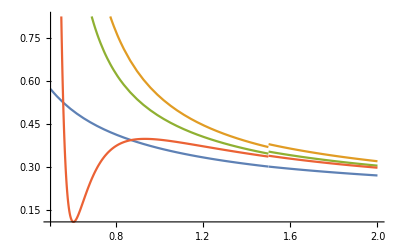

```mathematica
Plot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,2}]
```

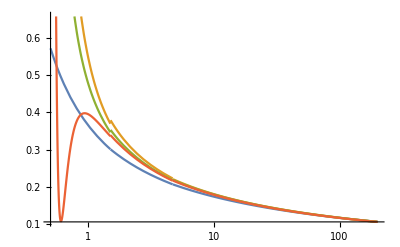

```mathematica
LogLinearPlot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,200}]
```

### μ

```mathematica
(* scale setting prescription: mu/mQ = fudge * alpha_s(mu), solved numerically for mu *)
```

#### LO

```mathematica
Clear[mu];
```

```mathematica
fudge=4;
```

```mathematica
(* Start Nf = 4 *)
```

```mathematica
Nf4α1Loopμ=Reverse@Table[Max[1,mu/.FindRoot[mu==fudge αs1Loop[mu]mQ,{mu,10}]],{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{4.05254,3.74331,3.42818,3.1062,2.77611,2.43616,2.08379,1.715}

```mathematica
Nf4α1LoopMid=Table[αs1Loop[Nf4α1Loopμ[[k]]],{k,1,Length[Nf4α1Loopμ]}]
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
Nf4α1LoopStepTab=Round[4/(.2 Nf4α1LoopMid^2)]
```

{430,411,390,367,342,314,282,245}

```mathematica
Nf4α1LoopBig=Table[αs1Loop[1/2Nf4α1Loopμ[[k]]],{k,1,Length[Nf4α1Loopμ]}]
```

{0.268835,0.276665,0.28589,0.296997,0.311546,0.330832,0.357283,0.396841}

```mathematica
Nf4α1LoopSmall=Table[αs1Loop[2Nf4α1Loopμ[[k]]],{k,1,Length[Nf4α1Loopμ]}]
```

{0.181799,0.185058,0.188807,0.193197,0.198453,0.204935,0.213849,0.226354}

```mathematica
Length[DeleteDuplicates[Join[Nf4α1LoopMid,Nf4α1LoopBig,Nf4α1LoopSmall]]]
```

24

```mathematica
(* Start Nf = 5 *)
```

```mathematica
Nf5α1Loopμ=Reverse@Table[mu/.FindRoot[mu==fudge αs1Loop[mu]mQ,{mu,10}],{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{83.1266,72.9651,62.6156,52.0329,41.1465,29.8326,17.822,4.05254}

```mathematica
Mt
```

173.34

```mathematica
Nf5α1LoopMid=Table[αs1Loop[Nf5α1Loopμ[[k]]],{k,1,Length[Nf5α1Loopμ]}]
```

{0.11989,0.122221,0.125074,0.128711,0.133637,0.141032,0.154751,0.21556}

```mathematica
Nf5α1LoopStepTab=Round[4/(.2 Nf5α1LoopMid^2)]
```

{1391,1339,1278,1207,1120,1006,835,430}

```mathematica
Nf5α1LoopBig=Table[αs1Loop[1/2Nf5α1Loopμ[[k]]],{k,1,Length[Nf5α1Loopμ]}]
```

{0.133418,0.136311,0.13987,0.144434,0.150667,0.160132,0.178055,0.268835}

```mathematica
Nf5α1LoopSmall=Table[αs1Loop[2Nf5α1Loopμ[[k]]],{k,1,Length[Nf5α1Loopμ]}]
```

{0.108852,0.11077,0.113109,0.116075,0.120067,0.126002,0.136841,0.181799}

```mathematica
Length[DeleteDuplicates[Join[Nf5α1LoopMid,Nf5α1LoopBig,Nf5α1LoopSmall]]]
```

24

```mathematica
Nf4α1LoopmQ=Reverse@Table[mQ,{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{4.7,4.24286,3.78571,3.32857,2.87143,2.41429,1.95714,1.5}

```mathematica
Nf5α1LoopmQ=Reverse@Table[mQ,{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{173.34,149.249,125.157,101.066,76.9743,52.8829,28.7914,4.7}

#### NLO

```mathematica
(* Start Nf = 4 *)
```

```mathematica
Nf4α2Loopμ=Reverse@Table[Max[1,mu/.FindRoot[mu==fudge αs2Loop[mu]mQ,{mu,10}]],{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{4.31311,4.00065,3.68202,3.35624,3.02203,2.67764,2.32054,1.94685}

```mathematica
Nf4mQTab=Reverse@Table[mQ,{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{4.7,4.24286,3.78571,3.32857,2.87143,2.41429,1.95714,1.5}

```mathematica
Nf4α2Loopμ/Nf4mQTab
```

{0.917683,0.942915,0.972609,1.00831,1.05245,1.10908,1.18568,1.2979}

```mathematica
2Nf4α2Loopμ/Nf4mQTab
```

{1.83537,1.88583,1.94522,2.01663,2.1049,2.21816,2.37136,2.5958}

```mathematica
1/2Nf4α2Loopμ/Nf4mQTab
```

{0.458842,0.471457,0.486305,0.504157,0.526225,0.554541,0.592839,0.648951}

```mathematica
Nf4α2LoopMid=Table[αs2Loop[Nf4α2Loopμ[[k]]],{k,1,Length[Nf4α2Loopμ]}]
```

{0.229421,0.235729,0.243152,0.252078,0.263112,0.277271,0.29642,0.324475}

```mathematica
Nf4α2LoopStepTab=Round[4/(.2 Nf4α2LoopMid^2)]
```

{380,360,338,315,289,260,228,190}

```mathematica
Nf4α2LoopBig=Table[αs2Loop[1/2Nf4α2Loopμ[[k]]],{k,1,Length[Nf4α2Loopμ]}]
```

{0.307437,0.319756,0.334731,0.353465,0.377818,0.404105,0.461228,0.564997}

```mathematica
Nf4α2LoopSmall=Table[αs2Loop[2Nf4α2Loopμ[[k]]],{k,1,Length[Nf4α2Loopμ]}]
```

{0.18711,0.190696,0.194827,0.199668,0.205469,0.212624,0.223621,0.238097}

```mathematica
Nf4α2LoopSmall[[-2]]=0.22362;
```

```mathematica
Length[DeleteDuplicates[Join[Nf4α2LoopMid,Nf4α2LoopBig,Nf4α2LoopSmall]]]
```

24

```mathematica
(* Start Nf = 5 *)
```

```mathematica
Nf5α2Loopμ=Reverse@Table[mu/.FindRoot[mu==fudge αs2Loop[mu]mQ,{mu,10}],{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{83.4672,73.3356,63.0103,52.4444,41.5642,30.2405,18.1903,4.31311}

```mathematica
Mt
```

173.34

```mathematica
Nf5mQTab=Reverse@Table[mQ,{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{173.34,149.249,125.157,101.066,76.9743,52.8829,28.7914,4.7}

```mathematica
Nf5α2Loopμ/Nf5mQTab
```

{0.481523,0.491366,0.50345,0.518914,0.539976,0.571839,0.631796,0.917683}

```mathematica
2Nf5α2Loopμ/Nf5mQTab
```

{0.963046,0.982731,1.0069,1.03783,1.07995,1.14368,1.26359,1.83537}

```mathematica
1/2Nf5α2Loopμ/Nf5mQTab
```

{0.240762,0.245683,0.251725,0.259457,0.269988,0.285919,0.315898,0.458842}

```mathematica
Nf5α2LoopMid=Table[αs2Loop[Nf5α2Loopμ[[k]]],{k,1,Length[Nf5α2Loopμ]}]
```

{0.120381,0.122841,0.125862,0.129728,0.134994,0.14296,0.157949,0.229421}

```mathematica
Nf5α2LoopStepTab=Round[4/(.2 Nf5α2LoopMid^2)]
```

{1380,1325,1263,1188,1097,979,802,380}

```mathematica
Nf5α2LoopBig=Table[αs2Loop[1/2Nf5α2Loopμ[[k]]],{k,1,Length[Nf5α2Loopμ]}]
```

{0.134898,0.138021,0.141879,0.146857,0.153712,0.164251,0.18467,0.307437}

```mathematica
Nf5α2LoopSmall=Table[αs2Loop[2Nf5α2Loopμ[[k]]],{k,1,Length[Nf5α2Loopμ]}]
```

{0.108756,0.110748,0.113181,0.116276,0.120457,0.126705,0.138215,0.18711}

```mathematica
Length[DeleteDuplicates[Join[Nf5α2LoopMid,Nf5α2LoopBig,Nf5α2LoopSmall]]]
```

24

```mathematica
Nf4α2LoopmQ=Reverse@Table[mQ,{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{4.7,4.24286,3.78571,3.32857,2.87143,2.41429,1.95714,1.5}

```mathematica
Nf5α2LoopmQ=Reverse@Table[mQ,{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{173.34,149.249,125.157,101.066,76.9743,52.8829,28.7914,4.7}

#### NNLO

```mathematica
(* Start Nf = 4 *)
```

```mathematica
Nf4α3Loopμ=Reverse@Table[Max[1,mu/.FindRoot[mu==fudge αs3Loop[mu]mQ,{mu,10}]],{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{4.24177,3.9304,3.61282,3.28803,2.95474,2.61112,2.2546,1.88115}

```mathematica
Nf4α3LoopMid=Table[αs3Loop[Nf4α3Loopμ[[k]]],{k,1,Length[Nf4α3Loopμ]}]
```

{0.225626,0.231589,0.238582,0.246955,0.257253,0.270383,0.287996,0.313525}

```mathematica
Nf4α3LoopStepTab=Round[4/(.2 Nf4α3LoopMid^2)]
```

{393,373,351,328,302,274,241,203}

```mathematica
Nf4mQTab=Reverse@Table[mQ,{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{4.7,4.24286,3.78571,3.32857,2.87143,2.41429,1.95714,1.5}

```mathematica
Nf4α2Loopμ/Nf4mQTab
```

{0.917683,0.942915,0.972609,1.00831,1.05245,1.10908,1.18568,1.2979}

```mathematica
2Nf4α2Loopμ/Nf4mQTab
```

{1.83537,1.88583,1.94522,2.01663,2.1049,2.21816,2.37136,2.5958}

```mathematica
1/2Nf4α2Loopμ/Nf4mQTab
```

{0.458842,0.471457,0.486305,0.504157,0.526225,0.554541,0.592839,0.648951}

```mathematica
Nf4α3LoopBig=Table[αs3Loop[1/2Nf4α3Loopμ[[k]]],{k,1,Length[Nf4α3Loopμ]}]
```

{0.296093,0.306917,0.319941,0.336039,0.34972,0.380431,0.426678,0.508047}

```mathematica
Nf4α3LoopSmall=Table[αs3Loop[2Nf4α3Loopμ[[k]]],{k,1,Length[Nf4α3Loopμ]}]
```

{0.187113,0.190693,0.194817,0.199654,0.205452,0.212612,0.221075,0.235162}

```mathematica
Length[DeleteDuplicates[Join[Nf4α3LoopMid,Nf4α3LoopBig,Nf4α3LoopSmall]]]
```

24

```mathematica
(* Start Nf = 5 *)
```

```mathematica
Nf5α3Loopμ=Reverse@Table[mu/.FindRoot[mu==fudge αs3Loop[mu]mQ,{mu,10}],{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{83.4695,73.3338,63.0043,52.434,41.5493,30.2209,18.1659,4.24177}

```mathematica
Mt
```

173.34

```mathematica
Nf5mQTab=Reverse@Table[mQ,{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{173.34,149.249,125.157,101.066,76.9743,52.8829,28.7914,4.7}

```mathematica
Nf5α3Loopμ/Nf5mQTab
```

{0.481536,0.491353,0.503401,0.518811,0.539782,0.571469,0.630948,0.902505}

```mathematica
2Nf5α3Loopμ/Nf5mQTab
```

{0.963073,0.982706,1.0068,1.03762,1.07956,1.14294,1.2619,1.80501}

```mathematica
1/2Nf5α3Loopμ/Nf5mQTab
```

{0.240768,0.245677,0.251701,0.259405,0.269891,0.285734,0.315474,0.451253}

```mathematica
Nf5α3LoopMid=Table[αs3Loop[Nf5α3Loopμ[[k]]],{k,1,Length[Nf5α3Loopμ]}]
```

{0.120384,0.122838,0.12585,0.129703,0.134945,0.142867,0.157737,0.225626}

```mathematica
Nf5α3LoopStepTab=Round[4/(.2 Nf5α3LoopMid^2)]
```

{1380,1325,1263,1189,1098,980,804,393}

```mathematica
Nf5α3LoopBig=Table[αs3Loop[1/2Nf5α3Loopμ[[k]]],{k,1,Length[Nf5α3Loopμ]}]
```

{0.134841,0.137946,0.14178,0.146722,0.153516,0.163936,0.184024,0.296093}

```mathematica
Nf5α3LoopSmall=Table[αs3Loop[2Nf5α3Loopμ[[k]]],{k,1,Length[Nf5α3Loopμ]}]
```

{0.108781,0.110771,0.113203,0.116293,0.120467,0.126701,0.138172,0.187113}

```mathematica
Length[DeleteDuplicates[Join[Nf5α3LoopMid,Nf5α3LoopBig,Nf5α3LoopSmall]]]
```

24

```mathematica
Nf4α3LoopmQ=Reverse@Table[mQ,{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{4.7,4.24286,3.78571,3.32857,2.87143,2.41429,1.95714,1.5}

```mathematica
Nf5α3LoopmQ=Reverse@Table[mQ,{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{173.34,149.249,125.157,101.066,76.9743,52.8829,28.7914,4.7}

### GFMC

```mathematica
datadir="~/Dropbox/heavy_quark_nuclei_BA/data/";
```

```mathematica
plotdir="~/Dropbox/heavy_quark_nuclei_BA/plots/";
```

```mathematica
NWalkers=200;
```

```mathematica
<<MaTeX`
```

```mathematica
markerlist={"□","○","△","▽","◇","▯","◦"};
```

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->None,RoundingRadius->0,FrameMargins->0.2,Background->Directive[Lighter[LightGray,0.75]]]
```

```mathematica
OLegend=LineLegend[{Directive[ColorData[97][1]],Directive[ColorData[97][2]],Directive[ColorData[97][5]],Directive[ColorData[97][3]]},{MaTeX["\\text{LO}",Magnification->0.8],MaTeX["\\text{NLO}",Magnification->0.8],MaTeX["\\text{mNLO}",Magnification->0.8],MaTeX["\\text{NNLO}",Magnification->0.8]},LegendMarkers->{Style[markerlist[[1]],1,Bold,ColorData[97][1]],Style[markerlist[[2]],1,Bold,ColorData[97][2]],Style[markerlist[[5]],1,Bold,ColorData[97][5]],Style[markerlist[[3]],1,Bold,ColorData[97][3]]},LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

```mathematica
OLegend2=LineLegend[{Directive[ColorData[97][1]],Directive[ColorData[97][2]],Directive[ColorData[97][5]],Directive[ColorData[97][3]]},{MaTeX["\\text{LO}",Magnification->0.8],MaTeX["\\text{NLO}",Magnification->0.8],MaTeX["\\text{mNLO}",Magnification->0.8],MaTeX["\\text{NNLO}",Magnification->0.8]},LegendMarkers->{Style[markerlist[[1]],1,Bold,ColorData[97][1]],Style[markerlist[[2]],1,Bold,ColorData[97][2]],Style[markerlist[[5]],1,Bold,ColorData[97][5]],Style[markerlist[[3]],1,Bold,ColorData[97][3]]},LegendLayout->{"Row",2},LegendMargins->0.5,LegendFunction->frame]
```

## Mesons

### a=0.2 dτ=0.2

#### QCD LO - HWF

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={430,430,430,430,430};
NWalkers=200;
Nf4α1LoopBig={0.21556,0.21556,0.21556,0.21556,0.21556};
aList={1,2,3,4,5};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
csvData=Table[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"],{xx,1,Length[aList]}]
```

({mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.020651606120431938, -0.020651606013590625, -0.02065160583817767, -0.02065160622101819, -0.020651605940787594, -0.020651606246151394, -0.020651606166876217, -0.020651606025844295, -0.020651605986578093, -0.020651606004794737, -0.020651606163699855, -0.020651605897513074, -0.020651606259209303, -0.020651606174485825, -0.020651606092189616, -0.020651606037606258, -0.020651606120781534, -0.020651606259509455, -0.02065160612469414, -0.020651606049131927, -0.02065160609026999, -0.02065160611135142, -0.020651606572442194, -0.02065160563225165, -0.020651605772783712, -0.02065160607346663, -0.02065160592664445, -0.020651605972895195, -0.020651606019117256, -0.020651605876553385, -0.020651606278458343, -0.020651606073471905, -0.020651605830316486, -0.020651606328862173, -0.020651606129004185, -0.020651605852897863, -0.02065160616125113, -0.02065160649905891, -0.020651606295083422, -0.02065160579070107, -0.020651605946710734, -0.020651605973202262, -0.020651605888370148, -0.020651606003158487, -0.020651605936987904, -0.0206516057210623, -0.020651606112032015, -0.020651605831228825, -0.0206516060097965, -0.02065160578698157, -0.02065160601659833, -0.02065160592377746, -0.020651605985655096, -0.020651606021544915, -0.02065160581406592, -0.02065160596939533, -0.020651606003662653, -0.020651605949793463, -0.020651605893809398, -0.020651605815749072, -0.020651605918701, -0.02065160608935031, -0.020651606073114545, -0.020651606059785825, -0.020651606144987282, -0.020651606024018748, -0.020651606151873725, -0.02065160597779786, -0.020651606045456874, -0.020651606008376778, -0.020651605899277285, -0.020651605900713174, -0.02065160575721751, -0.020651605998560727, -0.020651605692115105, -0.02065160598318741, -0.020651606234458948, -0.020651606222778094, -0.020651605989763254, -0.020651606248368218, -0.02065160593795202, -0.020651605977288816, -0.020651606132276238, -0.02065160600719677, -0.0206516059666903, -0.020651605889793742, -0.020651605943884217, -0.02065160611674034, -0.020651606208824166, -0.020651606095011377, -0.020651606236814155, -0.020651605386607395, -0.020651606297807882, -0.020651605990570268, -0.02065160594342584, -0.020651606033851334, -0.020651606022287192, -0.020651605820893162, -0.02065160586140409, -0.020651606110219472, -0.020651605919930743, -0.020651605965496388, -0.02065160599805387, -0.020651605942995428, -0.02065160596481844, -0.020651606126152557, -0.020651606099283324, -0.020651606122720927, -0.02065160596395122, -0.020651605988138953, -0.020651606018105846, -0.020651606089031715, -0.020651606159797085, -0.02065160594294932, -0.020651606036729497, -0.020651605858790875, -0.020651606082307573, -0.020651605991485848, -0.02065160593994642, -0.020651606250303187, -0.0206516059675632, -0.020651606179975024, -0.020651605958011052, -0.020651606210500644, -0.02065160603197096, -0.020651605986378437, -0.02065160594467966, -0.02065160620927467, -0.02065160596519349, -0.02065160604534553, -0.020651606085589167, -0.02065160608689232, -0.02065160615309572, -0.02065160597875603, -0.02065160610571259, -0.02065160591438282, -0.020651606352582556, -0.020651605950114393, -0.020651606111401922, -0.020651606013152076, -0.020651606003301338, -0.020651606177399785, -0.02065160603525961, -0.020651605789677917, -0.02065160613441383, -0.020651606218310144, -0.020651606223946385, -0.02065160588735399, -0.020651605988666288, -0.02065160609852174, -0.020651606016784826, -0.02065160623988901, -0.020651605986764215, -0.02065160599762769, -0.020651605925575616, -0.02065160599911796, -0.020651606002823824, -0.020651606035449813, -0.02065160595203106, -0.02065160625604144, -0.020651605893296537, -0.02065160618465503, -0.020651606222190234, -0.020651606104236227, -0.02065160604775004, -0.020651605947018422, -0.02065160607056158, -0.0206516060226754, -0.020651606080423122, -0.020651606063274833, -0.020651606160652956, -0.02065160608796155, -0.020651605775689884, -0.02065160609038395, -0.020651606037664423, -0.020651606051036202, -0.020651605938281848, -0.02065160585622875, -0.02065160569869042, -0.020651606219997502, -0.020651606015107543, -0.02065160606906294, -0.020651605990859207, -0.02065160596539757, -0.020651605942604147, -0.02065160609948562, -0.02065160598074164, -0.02065160608600705, -0.02065160623829089, -0.020651605467411814, -0.020651606065209768, -0.02065160586159597, -0.02065160612694806, -0.020651606121504105, -0.02065160611072408, -0.020651606163360474, -0.020651606219389853, -0.020651606019107985, -0.020651605916039862, -0.020651606007645058, -0.020651606164029262, -0.020651605690332565, -0.020651606137451917, -0.02065160629939263, -0.020651605954092756, -0.02065160618286661, -0.020651606213741534, -0.02065160592045048, -0.020651605951275485, -0.02065160599431423, -0.020651606186481732, -0.020651606144465675, -0.020651605763804433, -0.020651606075840743, -0.020651606315092812, -0.020651605732727216, -0.020651605961383202, -0.020651605962397814, -0.02065160598981138, -0.020651606265082514, -0.020651606409322096, -0.020651606107578213, -0.020651606015551067, -0.020651606468801844, -0.0206516058682068, -0.0206516058480906, -0.020651605842870485, -0.020651605863544878, -0.020651605860498332, -0.020651606233663473, -0.020651605962940064, -0.020651606054139526, -0.02065160614871089, -0.020651605709898085, -0.020651605914160084, -0.02065160600455321, -0.02065160602638839, -0.020651605883657834, -0.020651605945299138, -0.02065160586906466, -0.020651606224109477, -0.020651606107845406, -0.02065160585321512, -0.020651605937809934, -0.020651605944648953, -0.020651605984831217, -0.020651605750440033, -0.020651605981887387, -0.0206516059993781, -0.020651605929874955, -0.02065160592181054, -0.02065160591031905, -0.020651606164235177, -0.020651605972837418, -0.020651606124151626, -0.020651605903873178, -0.020651605909804725, -0.020651606013812863, -0.020651606573893973, -0.020651605990768988, -0.0206516060182455, -0.020651606059628673, -0.020651606045141217, -0.020651605975345908, -0.0206516059125474, -0.020651605480423326, -0.02065160587441279, -0.020651606314439325, -0.02065160570298115, -0.02065160601657944, -0.02065160608963958, -0.020651606201980217, -0.02065160621753358, -0.020651605874667203, -0.020651605782098053, -0.020651605794487708, -0.020651605874519682, -0.020651606265064144, -0.020651605923094604, -0.02065160612190229, -0.020651606201773736, -0.02065160594655529, -0.020651605827451704, -0.020651606183687332, -0.020651606399520916, -0.020651606225526416, -0.020651606059596237, -0.020651606069720704, -0.020651606061456256, -0.020651605899663014, -0.02065160612207125, -0.020651606089794064, -0.02065160675489172, -0.02065160603098117, -0.020651606180752572, -0.020651606520860875, -0.020651606472724283, -0.02065160561501369, -0.02065160590994224, -0.020651606096744986, -0.020651605887679784, -0.02065160609939316, -0.020651605918544612, -0.020651605837382205, -0.020651606126031473, -0.02065160630884141, -0.020651606230403404, -0.02065160619500241, -0.02065160594121364, -0.020651606197760665, -0.0206516061115175, -0.020651605764174318, -0.020651606023587555, -0.02065160655547432, -0.020651606267419593, -0.020651605386091114, -0.020651605994409145, -0.020651606086624183, -0.020651606200460637, -0.02065160611466152, -0.020651606079765884, -0.020651606075721494, -0.020651605940747293, -0.020651605924866572, -0.020651606029939314, -0.020651605943794348, -0.020651606257129695, -0.020651605900914614, -0.020651606030478754, -0.020651606105423465, -0.020651606283418517, -0.020651605786518572, -0.02065160600952191, -0.020651606399733655, -0.020651606067871555, -0.02065160587906677, -0.02065160579039246, -0.02065160610373093, -0.020651605901425237, -0.020651605973428428, -0.02065160575193911, -0.020651605946995426, -0.020651606039674354, -0.02065160587097908, -0.020651605973781254, -0.020651605932091754, -0.020651606002425694, -0.02065160605189316, -0.020651605887094915, -0.020651606073177283, -0.02065160599505216, -0.02065160608864785, -0.020651605992845545, -0.020651606155068662, -0.02065160636445512, -0.020651606101724278, -0.02065160599761195, -0.02065160583907464, -0.0206516057041347, -0.020651606072552543, -0.020651605965633757, -0.02065160577272178, -0.020651605907829745, -0.020651606041028028, -0.02065160590053861, -0.020651605978790566, -0.020651605899118335, -0.02065160615077354, -0.02065160617302105, -0.02065160595737888, -0.020651606250546933, -0.020651606331752195, -0.020651606476219057, -0.02065160579351623, -0.020651605468114276, -0.020651606208984, -0.020651606100045444, -0.020651605930875408, -0.0206516059435089, -0.020651606126629116, -0.02065160630875807, -0.020651605933707302, -0.020651605554254826, -0.020651606326921965, -0.020651605823560053, -0.02065160597027627, -0.020651606286080718],[2.3341491218520586e-10, 5.219316106082643e-10, nan, nan, 0.0, 3.300985344724431e-10, 3.300985344724431e-10, nan, 2.3341491218520586e-10, nan, 4.042864871490044e-10, nan, nan, nan, 3.300985344724431e-10, 2.3341491218520586e-10, 4.668298243704117e-10, nan, 3.300985344724431e-10, 3.300985344724431e-10, 3.300985344724431e-10, nan, 4.668298243704117e-10, 4.042864871490044e-10, nan, 2.3341491218520586e-10, nan, 4.668298243704117e-10, nan, 0.0, nan, 2.3341491218520586e-10, 0.0, 0.0, 5.219316106082643e-10, 4.668298243704117e-10, nan, 2.3341491218520586e-10, 2.3341491218520586e-10, 2.3341491218520586e-10, 3.300985344724431e-10, 5.219316106082643e-10, nan, 4.042864871490044e-10, nan, 0.0, nan, 2.3341491218520586e-10, 3.300985344724431e-10, nan, 3.300985344724431e-10, nan, 2.3341491218520586e-10, 5.219316106082643e-10, 0.0, 2.3341491218520586e-10, 3.300985344724431e-10, 0.0, 0.0, nan, 2.3341491218520586e-10, nan, 4.668298243704117e-10, nan, 2.3341491218520586e-10, 4.042864871490044e-10, 0.0, 4.668298243704117e-10, 0.0, 0.0, nan, 3.300985344724431e-10, nan, 4.042864871490044e-10, 0.0, 3.300985344724431e-10, 0.0, 0.0, 0.0, 3.300985344724431e-10, 2.3341491218520586e-10, 0.0, nan, 4.042864871490044e-10, 0.0, 0.0, nan, 4.042864871490044e-10, 0.0, 3.300985344724431e-10, 2.3341491218520586e-10, 5.71747433210298e-10, 3.300985344724431e-10, nan, 3.300985344724431e-10, nan, 3.300985344724431e-10, 3.300985344724431e-10, 2.3341491218520586e-10, 5.71747433210298e-10, 0.0, 4.042864871490044e-10, 2.3341491218520586e-10, 2.3341491218520586e-10, nan, nan, 0.0, 2.3341491218520586e-10, 3.300985344724431e-10, nan, 4.042864871490044e-10, 0.0, 2.3341491218520586e-10, 2.3341491218520586e-10, 0.0, nan, nan, 0.0, 0.0, nan, 4.042864871490044e-10, nan, nan, 3.300985344724431e-10, 2.3341491218520586e-10, nan, 0.0, nan, 3.300985344724431e-10, 0.0, 0.0, 0.0, 3.300985344724431e-10, 0.0, nan, nan, nan, 2.3341491218520586e-10, 3.300985344724431e-10, 0.0, 0.0, 0.0, 0.0, 0.0, 4.042864871490044e-10, 2.3341491218520586e-10, 2.3341491218520586e-10, nan, 2.3341491218520586e-10, 2.3341491218520586e-10, 0.0, 3.300985344724431e-10, 2.3341491218520586e-10, nan, 2.3341491218520586e-10, 2.3341491218520586e-10, 4.042864871490044e-10, 3.300985344724431e-10, 5.219316106082643e-10, 0.0, 4.042864871490044e-10, 2.3341491218520586e-10, 4.042864871490044e-10, nan, 4.668298243704117e-10, 3.300985344724431e-10, 4.042864871490044e-10, nan, 4.668298243704117e-10, 0.0, 3.300985344724431e-10, 2.3341491218520586e-10, 0.0, 0.0, nan, nan, 0.0, 0.0, 2.3341491218520586e-10, 3.300985344724431e-10, nan, 3.300985344724431e-10, 3.300985344724431e-10, nan, nan, 0.0, nan, 3.300985344724431e-10, 3.300985344724431e-10, 7.002447365556175e-10, nan, 0.0, nan, 0.0, nan, nan, 0.0, 3.300985344724431e-10, nan, 2.3341491218520586e-10, 4.042864871490044e-10, 3.300985344724431e-10, nan, nan, 3.300985344724431e-10, 2.3341491218520586e-10, 3.300985344724431e-10, 3.300985344724431e-10, 3.300985344724431e-10, 2.3341491218520586e-10, 3.300985344724431e-10, nan, 0.0, 3.300985344724431e-10, 3.300985344724431e-10, 2.3341491218520586e-10, nan, 0.0, 2.3341491218520586e-10, nan, 4.042864871490044e-10, 2.3341491218520586e-10, 3.300985344724431e-10, 4.042864871490044e-10, 4.042864871490044e-10, 0.0, 3.300985344724431e-10, nan, 3.300985344724431e-10, nan, nan, 4.668298243704117e-10, 2.3341491218520586e-10, 0.0, 0.0, 2.3341491218520586e-10, nan, 4.668298243704117e-10, nan, 0.0, 5.219316106082643e-10, 2.3341491218520586e-10, 3.300985344724431e-10, 0.0, nan, nan, 4.668298243704117e-10, nan, 0.0, 3.300985344724431e-10, 2.3341491218520586e-10, nan, nan, nan, nan, nan, nan, nan, 4.042864871490044e-10, 0.0, 2.3341491218520586e-10, 2.3341491218520586e-10, 0.0, 3.300985344724431e-10, nan, 0.0, nan, 2.3341491218520586e-10, 2.3341491218520586e-10, 3.300985344724431e-10, nan, 0.0, nan, nan, 2.3341491218520586e-10, 0.0, 0.0, nan, 2.3341491218520586e-10, 2.3341491218520586e-10, nan, nan, 3.300985344724431e-10, nan, 4.668298243704117e-10, nan, 0.0, 0.0, nan, nan, 3.300985344724431e-10, 2.3341491218520586e-10, 4.668298243704117e-10, 3.300985344724431e-10, 3.300985344724431e-10, 4.668298243704117e-10, 4.042864871490044e-10, 6.601970689448862e-10, nan, nan, 3.300985344724431e-10, 0.0, 2.3341491218520586e-10, 4.042864871490044e-10, 4.042864871490044e-10, 3.300985344724431e-10, 0.0, 0.0, 3.300985344724431e-10, nan, 3.300985344724431e-10, 2.3341491218520586e-10, 3.300985344724431e-10, 4.668298243704117e-10, 4.042864871490044e-10, 4.042864871490044e-10, 2.3341491218520586e-10, 2.3341491218520586e-10, 0.0, 2.3341491218520586e-10, 4.042864871490044e-10, 3.300985344724431e-10, nan, nan, nan, nan, nan, 0.0, 0.0, 2.3341491218520586e-10, 2.3341491218520586e-10, 3.300985344724431e-10, nan, 0.0, 2.3341491218520586e-10, 4.042864871490044e-10, 0.0, 3.300985344724431e-10, 4.042864871490044e-10, nan, 2.3341491218520586e-10, nan, 2.3341491218520586e-10, nan, 0.0, nan, 0.0, nan, nan, 2.3341491218520586e-10, nan, nan, nan, nan, nan, 4.042864871490044e-10, 4.042864871490044e-10, nan, 0.0, nan, nan, nan, 4.668298243704117e-10, 2.3341491218520586e-10, 0.0, nan, nan, 0.0, 2.3341491218520586e-10, 2.3341491218520586e-10, 0.0, nan, 4.668298243704117e-10, nan, 3.300985344724431e-10, nan, 4.042864871490044e-10, nan, 4.668298243704117e-10, 2.3341491218520586e-10, nan, 3.300985344724431e-10, 2.3341491218520586e-10, 0.0, 3.300985344724431e-10, 2.3341491218520586e-10, 3.300985344724431e-10],-0.0206516,2.72239×10^-9,-0.0395014}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.014885335254786223, -0.014837222787456746, -0.014739979314655993, -0.014700444412980736, -0.014807392417851662, -0.01491434729013699, -0.015041386610380932, -0.01513823424498445, -0.015293235515780905, -0.01575829177378143, -0.01543954035924385, -0.01525212003130381, -0.015407431550631992, -0.015340305518579718, -0.015149131577718489, -0.014968259244710817, -0.01525019127964982, -0.015290105950780808, -0.015293237647791133, -0.015234469878794983, -0.015324621693788858, -0.015197767884466409, -0.015520199581253892, -0.01517870244251811, -0.015208810197223617, -0.015193969673716253, -0.015150244097709186, -0.01502046266483873, -0.015234592380947739, -0.015263549099863064, -0.015369054812785679, -0.015310055188705925, -0.01535152917827562, -0.015317674384156585, -0.015322705862221652, -0.015514130050205544, -0.015214368255570078, -0.01549174903247017, -0.01567792006534651, -0.015861583265772673, -0.015709074632725403, -0.015422476423895414, -0.015570847100380359, -0.015813413699725918, -0.015747071186552497, -0.0154201731786023, -0.015488357635237485, -0.01526071158846166, -0.015194672481454062, -0.01543048168582937, -0.015364473945685549, -0.015509858502335728, -0.01539067054006286, -0.015542573814159358, -0.0154577119717281, -0.01535046269862834, -0.015468254725742087, -0.0154160842371965, -0.015101962263161559, -0.015160581030056559, -0.015148867958172371, -0.01510657285360722, -0.015000141301420196, -0.015053066532177046, -0.014953974019990704, -0.015001935194645736, -0.01509291687517958, -0.015222560226620585, -0.01520001628479638, -0.015232066861293931, -0.015187842394793727, -0.015002459830828376, -0.015081882355337374, -0.014986464499125484, -0.015070939315892084, -0.01513072403959392, -0.015122535262489748, -0.015115920729907925, -0.015230383696359734, -0.015209132758849598, -0.015418981938952636, -0.01531270595616783, -0.015402515552570445, -0.015269365543807046, -0.01520434657018362, -0.015156637722323153, -0.015278554715564222, -0.015274696073504948, -0.015402976357377656, -0.015571108769607317, -0.015490404298300611, -0.015371665166714291, -0.015494073616939802, -0.015641197611138562, -0.01590831614269126, -0.015927956086257505, -0.01631871837490848, -0.016072128192870433, -0.015937975456295633, -0.016010935583094424, -0.015876884031362934, -0.016115221839713555, -0.016077305225173106, -0.016063891542548423, -0.01618257968854024, -0.016401324542119552, -0.01639203765555865, -0.01635139752584725, -0.0163596769889173, -0.01625580611753445, -0.016546221696478722, -0.01669474909710078, -0.016538309009282184, -0.01672379729197651, -0.0164455986309222, -0.016932628121728202, -0.017510409000489082, -0.016860062986127432, -0.016766658404014208, -0.016884480994709163, -0.016820225738510258, -0.017302824306228683, -0.01752064691348009, -0.017056355588524898, -0.01730239599722245, -0.017316669118840375, -0.017855535199477496, -0.01836822562481483, -0.017953593077526735, -0.01753437247478622, -0.01761029712166333, -0.017642802985036714, -0.018289855555272114, -0.018138996844818324, -0.017626003835716483, -0.01733339109822429, -0.01721745989006071, -0.017077900202074354, -0.017134102649678375, -0.016956621725950933, -0.016723522909291622, -0.01638423965111649, -0.016305674060797512, -0.01625562883351253, -0.015998244050836635, -0.015798368180995163, -0.015816918444950347, -0.015830290148299144, -0.015807802293107995, -0.015951194508619523, -0.016065520205709772, -0.015916811856356065, -0.015901129066948745, -0.015819482028709173, -0.016132644919844424, -0.017499331388968094, -0.016788036288579316, -0.016330421804139145, -0.016206196036078074, -0.016247828145032162, -0.015783696976514296, -0.015580098096342396, -0.015536572862074507, -0.015883354258576888, -0.01601897281970101, -0.016028705217026516, -0.01578075888145465, -0.015786400249857228, -0.016198471011315205, -0.015995726443866196, -0.01611375474706644, -0.01607848646967118, -0.016543870497199596, -0.016364370627381015, -0.01606631346390814, -0.01598967353860946, -0.015975433249636194, -0.016084962115563404, -0.016492297766506046, -0.016566141879193128, -0.017165936698366687, -0.01660653121449089, -0.016567738405470586, -0.01649501877244677, -0.016285863565284844, -0.01633074246401964, -0.01623458869652954, -0.016187594004752046, -0.016488981677758592, -0.016431094031672772, -0.016786953536103044, -0.016864611372438366, -0.016777429429748622, -0.01680624422975581, -0.016523748303976606, -0.01659654487369877, -0.016585727119425204, -0.017047418688403475, -0.01678841541162366, -0.01711752532862057, -0.017450619686027517, -0.017258969077102827, -0.017292110783264526, -0.017460926267728855, -0.01727390831312929, -0.017645279424195547, -0.017848820945798174, -0.017741247674447676, -0.01798103787078415, -0.018229984778814975, -0.01762322275627934, -0.018048573905516486, -0.01805157801279749, -0.017941901121052487, -0.018368905993230072, -0.01895824289176219, -0.01839772994610145, -0.017945748438078328, -0.01825660778384582, -0.01793283342165784, -0.017795638326476546, -0.01785943893150896, -0.018364383703943676, -0.018544220838607378, -0.0184357650950198, -0.018080020040579216, -0.017909194740682765, -0.017573252983621824, -0.01762227280529077, -0.017461626017749053, -0.01742990543569326, -0.017148068678608516, -0.017038640881395034, -0.01724089785957305, -0.01730148204962594, -0.017976620693612035, -0.018168629833166042, -0.018345921421646476, -0.018383651132181517, -0.018167029710111738, -0.018068464105156206, -0.01802340811727266, -0.018373842380906377, -0.01900858817696045, -0.018989261781428915, -0.01938207694857874, -0.01785976253634543, -0.017589210138089412, -0.017312456252773525, -0.01710850145243088, -0.017057071072175918, -0.01736811670418317, -0.01720947856451178, -0.01731666892806055, -0.017536955667132578, -0.018914491658531398, -0.018787092160353087, -0.018962402266211136, -0.018995221754197093, -0.018144694328433172, -0.018157722225936757, -0.01826278381684286, -0.018393082429876396, -0.01830442465073913, -0.018568873840798972, -0.01974774387163532, -0.019039268581653432, -0.01890958437980631, -0.019386339852363703, -0.0193516457910791, -0.018917787130091058, -0.01933384979009233, -0.019148995420874223, -0.01869377802333815, -0.019135314102344033, -0.018769756776985586, -0.018770135351360243, -0.01827736263212341, -0.018426456657696325, -0.018513124934822593, -0.019185286138899117, -0.01829174097704505, -0.017989928578134785, -0.01818429124692653, -0.01818351708474823, -0.018148274670063642, -0.018100495525979525, -0.017793930489903544, -0.017701328212109547, -0.017547589678999054, -0.017626071409899562, -0.017660260426457144, -0.017758388818845464, -0.017807502701350803, -0.017573810274996406, -0.01788946624645407, -0.01829474132822729, -0.017923076085083034, -0.018487225602754818, -0.01862859300951769, -0.019305081222243753, -0.01884599130239583, -0.019074679543671882, -0.01895297626060056, -0.020071510749551796, -0.02144158568907355, -0.020951058447465823, -0.020133785710591056, -0.0201289695587232, -0.0201507397402713, -0.020811821650176508, -0.019946441159530343, -0.0208520657835188, -0.019268248569811946, -0.01867971415961108, -0.019724374536077116, -0.019278623433819312, -0.019298694909382855, -0.018941648749500013, -0.018408936210980078, -0.018609317199932973, -0.018281327022595783, -0.01783990053396066, -0.01790078177886842, -0.01769643777734375, -0.01765817873741887, -0.017533270996651, -0.017627781133387976, -0.017813970536731633, -0.017663263872305497, -0.017674402706128616, -0.018233550917897582, -0.018623185329411384, -0.018435221439148455, -0.018208719090993405, -0.018602357185294658, -0.01850797082573566, -0.018356621732130884, -0.017882201871703474, -0.01799564591897487, -0.01813244997199198, -0.01828990234374105, -0.018586660956092654, -0.018629263254437332, -0.018169183836417403, -0.0187717995309295, -0.018510942306215993, -0.018744949923549626, -0.01833141251084589, -0.018062530071756712, -0.01737460528377818, -0.01736392292130603, -0.017174534517351462, -0.016708755966244503, -0.016766797732826036, -0.01677407597892024, -0.016840142142102874, -0.01675898807482176, -0.016870918823731155, -0.01685732228495318, -0.016766634052370846, -0.016943455489531238, -0.016759127698453266, -0.0167817162522564, -0.01667736384156446, -0.01660398531339977, -0.016623660834390864, -0.016651103871800906, -0.016701039835415588, -0.016594039378660073, -0.016756593816540565, -0.016673249294371233, -0.017269700892531714, -0.01728917077916646, -0.01732537370299708, -0.01740681798949049, -0.017466856992459784, -0.01728808355934847, -0.017410679982027, -0.01743327735180215, -0.01736300900463284, -0.017390291355500364, -0.017486635793914497, -0.017198028649509388, -0.017521431681283173, -0.017654481528785092, -0.017545351008585237],[0.00047244156009392007, 0.00044466586524556385, 0.0004159792764019085, 0.0004013411807250966, 0.00041981836360996004, 0.00047370422131300506, 0.0005412400888860784, 0.000601668550821991, 0.0007736003579644495, 0.0011811236374714635, 0.0008067646238882335, 0.0005793900642139282, 0.0006428591607832184, 0.0005870361600206959, 0.0005486269040277976, 0.0005061339643561138, 0.0006712487719008557, 0.0007337864379899982, 0.0006404444468075032, 0.0005734055752471246, 0.0006114521140284456, 0.0006482698541501328, 0.0009042234454658348, 0.0005379005437433638, 0.0005265186709693163, 0.000498955270967432, 0.0004963814967045036, 0.0004661026260280829, 0.0005099337255056443, 0.0005393117490031905, 0.000582101230542491, 0.0005368209273384968, 0.0005470881152247386, 0.0005510226788494475, 0.0005777702075445945, 0.000646370354974317, 0.0005996660365696421, 0.0009005747090458086, 0.000954020725323339, 0.0009847749308598997, 0.000844077638435861, 0.0005795611695950413, 0.0006266472757274511, 0.0007250012633456185, 0.0006839701299946577, 0.0005422958754513172, 0.0005868263942756874, 0.0005227271053702605, 0.0005261030834793884, 0.000567231543835595, 0.0005306601258634081, 0.0005738541569153902, 0.0005662043963646156, 0.0006016248031031844, 0.0005448127509474524, 0.000511803981852148, 0.0005785949400541179, 0.000546057823615734, 0.0004586484705310237, 0.00047602876279617467, 0.0004946461707026531, 0.0004627487541908698, 0.00045169408181864495, 0.0004679155806749957, 0.0004498362393265182, 0.0004513526955172853, 0.0005000347841582339, 0.000532284986960949, 0.000477400905840368, 0.00047505489647144757, 0.00045686597455173536, 0.000424177814201406, 0.00043941166748613213, 0.0004207536123814388, 0.0004872074555403741, 0.0005149804111958741, 0.0004640162373700216, 0.00043895526375785116, 0.00045689785291476827, 0.00046733765750630246, 0.0005072628323597717, 0.00047193345058237974, 0.0004630132318367175, 0.00042666458021231227, 0.0004165447439582414, 0.0004007831983562245, 0.0004215541518811823, 0.0004401457324205212, 0.000446028990528497, 0.00048082765269756524, 0.0004830370952080127, 0.0004486700540044454, 0.0004923189020493139, 0.0005434050950016096, 0.0006171930064567656, 0.000596643753949318, 0.0008739122718995896, 0.0006570069681042273, 0.000563286524455958, 0.0005814644111284884, 0.0005474446057748341, 0.0006155640669351461, 0.0005944262307723648, 0.000617425851445898, 0.0006557032071388302, 0.0007169683458775541, 0.000736502113354213, 0.0007317655177729751, 0.0007260225312180876, 0.0007108405443468841, 0.0009227510591826689, 0.001048210673426536, 0.0009422606555016917, 0.0010102852135704878, 0.0008497916048321, 0.001077531267823445, 0.0013255830511556188, 0.0009533035545494628, 0.000908720269270693, 0.0009343685948149587, 0.0008897958780064712, 0.001052711041171567, 0.0013352021896177366, 0.0009923052342728233, 0.0012178288034132843, 0.001109346071695286, 0.0013375720151949117, 0.0015955279194477575, 0.0013639347190245238, 0.0009770608887250413, 0.0010002661307725441, 0.0010369463932488623, 0.0017396007106443082, 0.0016704225281223306, 0.00112231914055776, 0.00106702866467612, 0.0008952777990962666, 0.0008878934612242214, 0.0009470647479842624, 0.0008350794974613126, 0.00082975559627479, 0.0007082398424767545, 0.0007049689784983404, 0.0007289255871251448, 0.0006250682561400847, 0.0005967784441729459, 0.0006060781954349877, 0.000605301632450848, 0.0005945731228967668, 0.0006456872446175176, 0.0006984401844285914, 0.0006311384939314722, 0.0006412545553141391, 0.0006331255876003989, 0.0007709393725186196, 0.0018895739265419145, 0.0013068841306517684, 0.0009887557771141586, 0.0009560574359840958, 0.0009235327864906696, 0.0006576200908284537, 0.0006009779210531589, 0.0005321497840691664, 0.0006783718373178731, 0.000750830400297619, 0.0008455063074293787, 0.0006242736861452709, 0.0006830339373756815, 0.0008775403731268919, 0.0006681496476847052, 0.0006717573867576329, 0.0006778640567720513, 0.00097227901825353, 0.0008331508202994213, 0.0006900379862834188, 0.0006649009620987907, 0.0006277704797336706, 0.0006806239354789504, 0.000845171948880342, 0.0009479981361932148, 0.001617412444760886, 0.001065058765227708, 0.0009049080257671428, 0.0008261287134663782, 0.0006983652014356198, 0.000718614521460531, 0.0006680069945274009, 0.0006640967544472092, 0.0007953653406449082, 0.0007776705422680711, 0.000906435154091394, 0.0008998198235227436, 0.0008199378401659316, 0.0008928869615932079, 0.0007538635673654258, 0.0007629308768234049, 0.0007704741820357469, 0.0010130928756627302, 0.0008031704149189018, 0.0008728176134206523, 0.0010019320806492753, 0.0008804138183395609, 0.0009026992245307576, 0.0009140856178419976, 0.0008845661800508656, 0.0010409103585577622, 0.0010926224371194159, 0.0009916497114038669, 0.0010527771483176676, 0.0011515806469234537, 0.0009061753862913213, 0.0010103537954379586, 0.0010313105713662262, 0.0010844069794721872, 0.0013527192439842968, 0.001685375862791149, 0.0012162440568982706, 0.00104681789529114, 0.0011465640920521809, 0.0010346936061589752, 0.000989758389503696, 0.0010404213540184885, 0.0012756962576015141, 0.0013861817261023085, 0.0014222710297815437, 0.0012129634532271995, 0.0009574737203474423, 0.0008435806541840646, 0.0008563035947603053, 0.0007911417012657118, 0.0008047886106967689, 0.0006806086137681068, 0.000687421145315873, 0.0007545112008201866, 0.0007843463831261064, 0.0011059247416877673, 0.0011569490378686733, 0.0011580350688144923, 0.0010381123286296841, 0.0009759486649064267, 0.0009401010457373817, 0.0009261027137161366, 0.0011264084186761733, 0.0012842105161864127, 0.0013629953145078526, 0.0019395774937441314, 0.0009355651863855992, 0.0008229948714655821, 0.0007419864118953995, 0.0006707677015404947, 0.0006567943043109907, 0.0007222714961289236, 0.0006972106230914468, 0.0007498723775994623, 0.0008390870208598082, 0.0018495854949047692, 0.0014583922762142795, 0.0015195663166261244, 0.0015843266630603849, 0.0010241824896006007, 0.0009180544350217746, 0.0008743366134923519, 0.0009661138506172158, 0.0009545572049182832, 0.0010311910429412026, 0.001546404978382681, 0.0011475873871399618, 0.0010998567990874997, 0.0012790181209563416, 0.0011925533340850303, 0.001035793130583945, 0.0012017954867621706, 0.0011542871157743536, 0.0010386316479901463, 0.0012727389653055365, 0.001155921833383268, 0.0012386244761969935, 0.0009227298478101076, 0.0009751950521681487, 0.001104125019874631, 0.001822962619611564, 0.0012104333197492832, 0.0010485332406415973, 0.0011741061603798807, 0.0012385631387021102, 0.0011603899597076026, 0.0011315337998643058, 0.0011060501664033212, 0.0009764174093420249, 0.0009146529814039971, 0.000911156932160136, 0.0009402011866646829, 0.0009913976511331973, 0.0010054631971283718, 0.0009499919980030963, 0.0011162734158443554, 0.001267504553085038, 0.0010522547142347942, 0.0012687223643542056, 0.0012741793682144484, 0.0016326819906737119, 0.001387309076335551, 0.0014542266186329444, 0.0015108134582710315, 0.0021835524219555365, 0.0031279060758395956, 0.00237195376192854, 0.0019362968332202735, 0.0018737432314287724, 0.0018035075961518592, 0.0023206666878739434, 0.0019052726027983138, 0.0027416766934228666, 0.001627558744169251, 0.001350505652234643, 0.0020199327664303154, 0.0015843782476746995, 0.0016058333966443143, 0.0015649909809277234, 0.0012621348039728508, 0.0015983673294585857, 0.0014181299707388343, 0.0011452917531973772, 0.0011327696314035473, 0.0010182239076114005, 0.0009740225156481237, 0.0009058964703593717, 0.0009198826587679878, 0.0009664535707805842, 0.0008941892050196703, 0.0009632422480598685, 0.001154190944201999, 0.0013142739849882298, 0.0012460707750320923, 0.0011269708827917311, 0.001208139259054212, 0.001165287713389701, 0.0011643235914610443, 0.0009678478035038617, 0.0009678928028175882, 0.000993191407098224, 0.001054989409822313, 0.0012120200973017485, 0.0012491501672632218, 0.0010757872391997235, 0.0014981238984534575, 0.001287887236146612, 0.001508939838137204, 0.0013576016891912234, 0.0012693448282035918, 0.0008937405848558516, 0.0009118697156389348, 0.0008537511026891661, 0.0007006603438530334, 0.0007039762667542371, 0.0006685687513922321, 0.0007022576733572173, 0.000674945863786903, 0.0007625001186542345, 0.0007620895856168815, 0.0007172651767453445, 0.0008424114418780468, 0.0007203916472758703, 0.0007047962177918506, 0.0006643410288715776, 0.0006110761892566088, 0.0006132851851952257, 0.0006308087144922383, 0.0006042789233680989, 0.0006143771634524421, 0.0006846559839618578, 0.0007103783896074138, 0.0010118673685199826, 0.0009624110472023989, 0.0009333302960993184, 0.0009192278444698221, 0.000941673483026178, 0.0008730516296021865, 0.0009684956778196418, 0.0009372789994282755, 0.0008291323093465955, 0.0008899359265944262, 0.0008721379597587201, 0.000813857874432846, 0.0009720207159661249, 0.0010601365271424251, 0.001056171356552937],-0.0135861,0.000179878,0.343337}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.010279588291747082, -0.010356478051643369, -0.010391724990956567, -0.010442219320114732, -0.010453043063915375, -0.010437564845115996, -0.01052443113720345, -0.010462466871765967, -0.010412215372748695, -0.010509417062980267, -0.010553246244567964, -0.010510060588024105, -0.010570257215593779, -0.010464825655723152, -0.010406039599679002, -0.010328301477110037, -0.010442126026663428, -0.010428918109655252, -0.01043300176125205, -0.01048577057266529, -0.01056324773839149, -0.010514649396484553, -0.010593109680860505, -0.010533411358602283, -0.010687949643098932, -0.010689720373730697, -0.01061814036597129, -0.010599735366060157, -0.010643284299197994, -0.010720100851158642, -0.010748204793431297, -0.010939884463364634, -0.010935846052485166, -0.010982481097939248, -0.010964321939426154, -0.011029011757837102, -0.010943530792721692, -0.010916905907459936, -0.010932453724340539, -0.010923473849677548, -0.011012559915441499, -0.011076427487240663, -0.011242436181696907, -0.011238281582612362, -0.011147932193960007, -0.01128792038687673, -0.01141679874257503, -0.011577596349622056, -0.011539111380743771, -0.011690479500649765, -0.012079951066674364, -0.012153007703162093, -0.01227730372671605, -0.012123229546143638, -0.0119770397863683, -0.01229415760371171, -0.012582594321269703, -0.012174307781155592, -0.012234691920809922, -0.012280340189478897, -0.012543192047665323, -0.013064215747268347, -0.012587297080316327, -0.012384550872407135, -0.012685182666082269, -0.012798910384406129, -0.012249019456991805, -0.012843771642449545, -0.012598048359530845, -0.012839343935445285, -0.01244961940995977, -0.012119661186374071, -0.011800713737718493, -0.011827936288040396, -0.011643741946615634, -0.011984897107763594, -0.01208184683173618, -0.012302117865538517, -0.012563612689167216, -0.012668879715772125, -0.012948047257127665, -0.014947295510986518, -0.013255161437600749, -0.012498790546493003, -0.012503099410353597, -0.012780944500342534, -0.012395003114317689, -0.012346586073062183, -0.012753567409369806, -0.012765269543140214, -0.012339967921462512, -0.012533057787214977, -0.012582820749367413, -0.012542378406634863, -0.012791405859451361, -0.012662403221597368, -0.012492922910663961, -0.012619324627040778, -0.012623998437803869, -0.012888602628363005, -0.012690034834398263, -0.01281837521522324, -0.013214028935403615, -0.014606306858857547, -0.014028213716933977, -0.0140533877025921, -0.013622161672155313, -0.013486883376615123, -0.014382876757969542, -0.012983301928702928, -0.01256291540877931, -0.012774787735591228, -0.012968480424255243, -0.013809995060976226, -0.013030735329062404, -0.012607900076210769, -0.012879544094645246, -0.012988764665063194, -0.01311719585779607, -0.012763161384367843, -0.014645762836156283, -0.012565448138008644, -0.012904378476356445, -0.013323419475061217, -0.014601707460206122, -0.013476414449288286, -0.01299456340734501, -0.012838231451369706, -0.012419995044422625, -0.012199391391280096, -0.01205938144741014, -0.012221041081175384, -0.012777867606218725, -0.0129767845884432, -0.012948467654828431, -0.013049499510666236, -0.012543826219550209, -0.012442593270819811, -0.012633732009902254, -0.012355549229858936, -0.012293918299848269, -0.012294036396785401, -0.012159119069465867, -0.01209797600921679, -0.012269950271141606, -0.012390723630337972, -0.01220110801027825, -0.012203697576239217, -0.012212722527869941, -0.012112968550461317, -0.012251867315291378, -0.012140526739258214, -0.012287094047399715, -0.012230929519822444, -0.012100949641796057, -0.012074293572622142, -0.012075240786875047, -0.011992467819876248, -0.011875798890535418, -0.011708285550307186, -0.011600423087408926, -0.011701961100848686, -0.011599795774826324, -0.011629599917723048, -0.011840171425694294, -0.012053997399348643, -0.012262298206971152, -0.012008909356976053, -0.012127538667209337, -0.012292443381382938, -0.012189851847430594, -0.012146087080573919, -0.012185115135596166, -0.012056437128668667, -0.011962016009965402, -0.011852455217644168, -0.01190432667350003, -0.01177544662918785, -0.01183866564246716, -0.01187177914096653, -0.011946483376521032, -0.012084825864193053, -0.012226609494601805, -0.01208148112853035, -0.011864102197303696, -0.011831397930973809, -0.01216020978897583, -0.01194514262120529, -0.012111990652474177, -0.012129240026749253, -0.012730722553036223, -0.014721458242495584, -0.01314228896684958, -0.012605669436857295, -0.012533095581211125, -0.012523357550794884, -0.012547146796219716, -0.012532749482073797, -0.013080495112222014, -0.013316890026664608, -0.013099890963956444, -0.01329731376739248, -0.012848557347966033, -0.013085348474422488, -0.01300952593745214, -0.013586653305640298, -0.013305614779145067, -0.013560637558456183, -0.013621265661609032, -0.0137521129495337, -0.013426460753232372, -0.013378382922565067, -0.013602028240749948, -0.013225776949735925, -0.013017387515149002, -0.013291033139560404, -0.012960994452291775, -0.012685695680365762, -0.01275133610739212, -0.012762570228126218, -0.012621231616142604, -0.012420544009460945, -0.012305175180894447, -0.012192654593544556, -0.012234196801636276, -0.012326626521455431, -0.012315484626796802, -0.012289013636094715, -0.01232961949998717, -0.012540796865342579, -0.012731508926469685, -0.012959470338328349, -0.012926469694707865, -0.013027668988033585, -0.012811778739115473, -0.012750571704768785, -0.013017248492630301, -0.012936733612472716, -0.013057105119938716, -0.013106724056752577, -0.013031312654204694, -0.013290042862903024, -0.013247945845897963, -0.01318208852246878, -0.013159483479677268, -0.013157151741347328, -0.012984186662533237, -0.01299965529487683, -0.012981080084651085, -0.012915933216648169, -0.012951908005786049, -0.013010391019223789, -0.01288098271312823, -0.012977197905600975, -0.012900469992453848, -0.013016856621364552, -0.012969868857617521, -0.01304908955627505, -0.012957562399034854, -0.012920067221500657, -0.013042021645502918, -0.013160817322919266, -0.013147314962640945, -0.013285166212463185, -0.014286283293722501, -0.01721039060192903, -0.014211383589434154, -0.013316259631769203, -0.01374776943230265, -0.013920200248142238, -0.013848005955986635, -0.014592175419100675, -0.013681780982440212, -0.0134800215979466, -0.013477277323772163, -0.013279651290664336, -0.013200588775879046, -0.01343879178849507, -0.013260965243852483, -0.012973858632355567, -0.01299487037018098, -0.013018728418500125, -0.012984678107207638, -0.01305548042957436, -0.013102597670732517, -0.013115289838542927, -0.013187120130583537, -0.012942889616566047, -0.01293687799287636, -0.012855307926625054, -0.013049740168911103, -0.013017575934669396, -0.013097533862304651, -0.01377018413975272, -0.01368720865318604, -0.01389983998366716, -0.013937506282068088, -0.01382150765891187, -0.013435032453520228, -0.013706509472562158, -0.013900635925089267, -0.013751398131400019, -0.013855198742954869, -0.013781401880796112, -0.01361016366404388, -0.0139758186929408, -0.014544598325869183, -0.01408037862692227, -0.014153169067886072, -0.014270391845841281, -0.013814358207094568, -0.013828102643631705, -0.013754687498931556, -0.01367051043527006, -0.013693220154927795, -0.014004364228777443, -0.014126000098291675, -0.014137587796055692, -0.014095352150833866, -0.014315536792099468, -0.014101651530242357, -0.01394696929560867, -0.013647151611705202, -0.013749063561069584, -0.014080088992186164, -0.014228902486853998, -0.014060758245559586, -0.014031240784527175, -0.013992277470550617, -0.014015704507843618, -0.014351604763521411, -0.014277738025222742, -0.014360809219657107, -0.01582255802850066, -0.023739605509808175, -0.015171249922014402, -0.014356831111892206, -0.014666290697023809, -0.01418947530610661, -0.014391564030103084, -0.014074662704971982, -0.014452304887839013, -0.014156554951535786, -0.014017718732778147, -0.014380847589613194, -0.014011176035132427, -0.014149490357705432, -0.013898130064845525, -0.013706143554406362, -0.01377369875130052, -0.013699857058759013, -0.013436126116002891, -0.013734063724426692, -0.013514852736272755, -0.013867521724094434, -0.014169745731107597, -0.014043422841936127, -0.013850195504372323, -0.014019548145942185, -0.013659173567412709, -0.01359079026007759, -0.01370607882240846, -0.013934790709634068, -0.013720504116058942, -0.013895886452813663, -0.013812364902661743, -0.013787817439324196, -0.014083742381635145, -0.014131662812890433, -0.014075614701197555, -0.013974503954736803, -0.013918739656401795, -0.014105291886820257, -0.013982583638203367, -0.01386595503936249, -0.014107556084634484, -0.014189431179027587, -0.014315468448077361, -0.014280321844574909, -0.014396298795699675, -0.014321062870966756, -0.014225983242066823, -0.014628176257968516, -0.015020234301593677, -0.015412725787900311, -0.014997722805702305, -0.01485706055750932],[0.00034968389335872634, 0.00036643175042364213, 0.0003714515503334991, 0.00039717737178766535, 0.0003866903417112702, 0.0003857487908005574, 0.0004175865759742136, 0.00039459731451292244, 0.00038264826608472356, 0.0004251633069399274, 0.00045350319972128477, 0.00043068833231793113, 0.00046704879124949905, 0.0004131176399526134, 0.00038882852365849127, 0.0003762232075635155, 0.0004034742701423212, 0.00039385495098105835, 0.00038041288929843313, 0.000386530919102621, 0.0004061882928607234, 0.0003818381798167774, 0.0004073029742914482, 0.00038474810633099595, 0.00041984672022117646, 0.000413094837205968, 0.00038604600108366665, 0.0003816210808229886, 0.0003864321454015605, 0.0004130617310318704, 0.0004164979817973523, 0.000473052152793258, 0.00046795124656174946, 0.0004883811234602773, 0.0004818321152363752, 0.0005100197201065189, 0.0004987536604128218, 0.00048458212201215646, 0.0005068060847396747, 0.00049137027052788, 0.0005158728654021222, 0.0005183839127343898, 0.0005719605830703205, 0.0005451130609705869, 0.0005105450931033015, 0.0005452667074075571, 0.0005851426671730942, 0.0006289913950586503, 0.0006257974556179781, 0.0006758787787866378, 0.0008326631647154977, 0.0008716063242381103, 0.0009797610695926012, 0.0008548523049757936, 0.0007648392970683751, 0.0009171528862936838, 0.001089982614940177, 0.0009002752304078112, 0.0009264710384149662, 0.0009534581870820322, 0.00106706287080687, 0.0013348561879362665, 0.0012044527470841712, 0.0011108776726282308, 0.001275280273900085, 0.0013611789652784665, 0.0009764529097702857, 0.0012945875621329123, 0.0011320124202342547, 0.0012845164843874445, 0.0010362902466920251, 0.000861282606352131, 0.0007183601035436096, 0.000710618470887382, 0.0006684020045278671, 0.0008144162454324683, 0.0008755126934128366, 0.0009824818462087215, 0.0011023114176188728, 0.0011566513809095735, 0.0012865754058740014, 0.0031704155086935476, 0.0015762418867784633, 0.0012040007122528602, 0.001171681425430445, 0.0013306540550467258, 0.0010366316279590351, 0.0009689141685562502, 0.0012140820428979562, 0.0012281762819254494, 0.0010133551698574149, 0.001093396262609265, 0.0010970605702464028, 0.0010513703029698819, 0.001181089082816616, 0.0009676119632759834, 0.0008910508617770243, 0.0009471530508999715, 0.0009938918563163336, 0.0011990317655361862, 0.0011214948000412975, 0.001146602067960214, 0.0013216660790914235, 0.002414128795943413, 0.001963123805277841, 0.0020740989220611327, 0.001715594366968677, 0.0017842136298511096, 0.0027597524394343867, 0.0014995422220509722, 0.001080108801710882, 0.0012328349869341047, 0.0014762275571707324, 0.002211241382102408, 0.0014639901672865855, 0.0010834875908061032, 0.0012715322830612451, 0.0013096549726316967, 0.001370880324464989, 0.0011424780258825966, 0.0028765879427534867, 0.0010635806559416898, 0.0013184719486904874, 0.0016965192966537069, 0.00278911002600564, 0.0017426724434466642, 0.0013582933847647858, 0.0011857283294617505, 0.0009200857139688776, 0.0008002482731413521, 0.000722879380865135, 0.0007845099066173908, 0.0011550634373597957, 0.00120672104478334, 0.0011723788154910711, 0.0012728170976138004, 0.0009062807349603498, 0.0009114110094803948, 0.0010358101045683458, 0.0008734936221537181, 0.0008201771454634034, 0.0008105252426080725, 0.0007650643425018349, 0.0007217879918544831, 0.0007611854682626801, 0.0008465538736378677, 0.0007860627047678858, 0.0007804167039421253, 0.0008180079941481436, 0.0007933911315063005, 0.0008441634558438276, 0.000821519274867444, 0.0008977191851741672, 0.0008629441504362594, 0.0007436504877595305, 0.000759170252698177, 0.000817614310796596, 0.0008117187693341586, 0.0007097025803648738, 0.0006439756600442314, 0.000613190703468995, 0.0006825592821587758, 0.0006501115025095938, 0.000638197587795839, 0.000691655424833233, 0.0007835743925376914, 0.0008833621476272856, 0.0007674751920652658, 0.0007732518910429152, 0.0008232594608343606, 0.0007674901834817445, 0.0007433023631821253, 0.0007313183939070559, 0.0006694954302961538, 0.0006324038126981002, 0.0006004974773648795, 0.0006318504655384058, 0.0006009246072277041, 0.0006058167622795937, 0.0006131312938896284, 0.0006766101470515479, 0.0007636702000598873, 0.0008062302166075849, 0.0007412669961568094, 0.0006324894329137105, 0.0006095983681275081, 0.00075233667432277, 0.0006726756280601277, 0.0007925453812351074, 0.000823090228018382, 0.001273241924414296, 0.003068740060617675, 0.0015634892308500387, 0.0010692845633377512, 0.0010967190381836699, 0.0009906451997829203, 0.0010390775237468614, 0.0009499595888167853, 0.0011417942527322666, 0.001288008355834339, 0.001092706448469668, 0.0012200994897636455, 0.000967770821295019, 0.001118191280824067, 0.001130253397799591, 0.001606161027234601, 0.0015295537038599533, 0.0016447125448518613, 0.0014806260585115826, 0.0015986790117123123, 0.0015462750666017423, 0.0015391228821186897, 0.0016725149264107005, 0.0014800606638265459, 0.0013456189173792325, 0.0015218699333350296, 0.0011674315490642977, 0.0009970767317742603, 0.0010165163863289888, 0.001049556139392021, 0.0009305853484206474, 0.000844559098785884, 0.0007962631747179367, 0.0007182796526542261, 0.0007394621641340574, 0.000812169900899759, 0.0007941246076337053, 0.0007548943206161197, 0.0007564940103369757, 0.0008409172326301974, 0.0009009785158842913, 0.0009264698628873091, 0.0009180932298638453, 0.0009298839347798265, 0.0008078028692441674, 0.0007654878313551906, 0.0008739568937203888, 0.0008287548864543112, 0.0008238843711656921, 0.0008572938771384048, 0.0008161159642685331, 0.0008960108095161832, 0.0008785958889808635, 0.0008161781616945698, 0.0008120890207751796, 0.0008116044395981237, 0.0007452530182664172, 0.0007683178828883936, 0.0007894604574870928, 0.0007536672418845108, 0.000760495744750991, 0.0007683739740663525, 0.0007304225820665503, 0.000751250688875368, 0.0007402721684845175, 0.000773013281920071, 0.0007566347994552629, 0.0007640603634804375, 0.0007149220544979403, 0.0007491198217043527, 0.0007718675725630602, 0.0008233355150248002, 0.000912236892733269, 0.0010099095795623014, 0.0018967997604876217, 0.004480360076647564, 0.0016764349619389563, 0.0009780732721026445, 0.0013352161585471814, 0.0014755117496995458, 0.0012863483967398021, 0.0019476325576105672, 0.001140488892504562, 0.001028069367810803, 0.0009819086921216934, 0.000869146778997063, 0.0008047076583703439, 0.000909028781728996, 0.0008730452391731066, 0.0007314589628716571, 0.0007322609838059788, 0.0007539617852159159, 0.000736153960233934, 0.0007420129705328883, 0.0007605139527163865, 0.0007515137981392149, 0.0008116118507811754, 0.0007486576276476043, 0.0007980924140897134, 0.0007931461582408653, 0.000964814035330115, 0.0008842681612796767, 0.0008791994908684409, 0.0015010448042578491, 0.0014738862735896871, 0.0016213415117327687, 0.0017078242677189776, 0.0015362845312219622, 0.0011403381499514593, 0.0013639356268194886, 0.0015022070125776327, 0.0013347269727258426, 0.0014475122156303577, 0.0013090044877800005, 0.0011119921335488768, 0.0013454996458555067, 0.0018715892444946351, 0.0012439906994996342, 0.0012050056432887995, 0.0014032353572074104, 0.0011433767822550775, 0.0010952113923844338, 0.0010677362326713812, 0.001019395302985774, 0.0010159848644729311, 0.0011217937836821988, 0.0011307379524934538, 0.0010981345297657174, 0.00108124448358188, 0.0010996525765877654, 0.0010222659182642924, 0.0009284767449643266, 0.0008332875281883789, 0.000857575228818199, 0.0009539081255148253, 0.0010040455073703877, 0.001036039064830684, 0.000952858937946714, 0.0009715358523303428, 0.0009907422869023137, 0.00130166943201477, 0.0012785991106561384, 0.001367895069484077, 0.0026434266888159075, 0.010395359088101954, 0.0022751804939248666, 0.0013950357850294971, 0.00155949063814139, 0.001152410982133056, 0.0013028694938947132, 0.0011261537107019892, 0.0013238685511148362, 0.0011586510844557715, 0.0010958818878294434, 0.001323430171950604, 0.0009978376895853492, 0.0011142631846402051, 0.0009818373981862806, 0.0009471912935331751, 0.000953858272651876, 0.0009346343661197675, 0.000867325945202261, 0.0009853792486090524, 0.0008800303201558113, 0.0010310906493552878, 0.0011894203070275733, 0.0011709195897116568, 0.0010477992441186462, 0.0011401500453926078, 0.0009175291341766456, 0.0008915501676441961, 0.0009380551957278334, 0.0009734359213722674, 0.0008747966685023601, 0.0009504054420009064, 0.0008975162627161117, 0.0009137156715868013, 0.00111382944941251, 0.0010334360578914772, 0.0009483750480732955, 0.0009346547223989593, 0.0008709757294613327, 0.0009183441589736539, 0.0008754319220897592, 0.0008346101737033175, 0.000945071577843957, 0.0009426623581790984, 0.0009845561272506782, 0.0010268720452162126, 0.0010857186933706984, 0.0010393832465544538, 0.0010802437667981892, 0.0013285578002433858, 0.001801477018292445, 0.0022061914999364825, 0.0018569206984630341, 0.0016085646166161427],-0.00953158,0.000182188,0.184346}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.009256966271019516, -0.009290567050246628, -0.009303282723475038, -0.009379346028484628, -0.009342195078722047, -0.009273581008807591, -0.009407465144037229, -0.009442522930959816, -0.009378289585084961, -0.009412130369944899, -0.009414047736703362, -0.00938936514083709, -0.009530196040900378, -0.009931102844617994, -0.009539455917053007, -0.009683527244537088, -0.00990216013489852, -0.01055115202353966, -0.010343538341804612, -0.010012623998951985, -0.009723842526303619, -0.00962806636599852, -0.009505257489100022, -0.009518981543893074, -0.00969400677752754, -0.009721507787711666, -0.00974739375567904, -0.009976062704071744, -0.009933491002347753, -0.010610601553193258, -0.010455569805299126, -0.01069094068024962, -0.010286633907078473, -0.010019092338673196, -0.009777308338548603, -0.009721050046796015, -0.00964076512331202, -0.009564841615898281, -0.009582879386523782, -0.009594284914679722, -0.009603211844648508, -0.009465372762390956, -0.00943230270733752, -0.009540893125173946, -0.009470382195560994, -0.009389408899368781, -0.009436893358264567, -0.009349895039375555, -0.009288550673091948, -0.009304497708068295, -0.009352043205209007, -0.009358045540441368, -0.009347818382777994, -0.009498481312923182, -0.00947271700645707, -0.00947614848311509, -0.009540343150327387, -0.009431746790141637, -0.00941146364834901, -0.009395259777012915, -0.009425566327273543, -0.009497610921533091, -0.009410607469765514, -0.009405807954434704, -0.009433685086860903, -0.009462850259266813, -0.009494736587891472, -0.00951390116705872, -0.009483934436929338, -0.009515672684638361, -0.00954028814872877, -0.009455040139980199, -0.009446664405346692, -0.009455784858553732, -0.009374692253222223, -0.009428458064474564, -0.009486400226376172, -0.00960453870859595, -0.009584231490122781, -0.009527006966219373, -0.009493320823975991, -0.009465732848367152, -0.00959236756635378, -0.009456827610068533, -0.009454984173818312, -0.00947857924960406, -0.009576576742805284, -0.009532289894471259, -0.009659258090906165, -0.009684182651327585, -0.009669286633542976, -0.009724440928508995, -0.009817356600201702, -0.009828489252329651, -0.009863775878687168, -0.009891513675879168, -0.009992596858597477, -0.00992040398357476, -0.009892029420469142, -0.009775494816339655, -0.009707998463407209, -0.009774050253616728, -0.009797157309455394, -0.009794133724571224, -0.009833403408026414, -0.009852713399327822, -0.010024788832753555, -0.009915905369062929, -0.009965340077143054, -0.009940209178541774, -0.009887760530106855, -0.009885250333840523, -0.00976210680608725, -0.010038356992120764, -0.009912838548632513, -0.009831991012600644, -0.009790590066293818, -0.009738233948428668, -0.00967479699886477, -0.00974249504732581, -0.00981757614022308, -0.00967241630345117, -0.00974001625398494, -0.009801657166436883, -0.009867467991077223, -0.00978450045770579, -0.00984959298472695, -0.009974320166563508, -0.010011526013635261, -0.010073721122782453, -0.010073431778950656, -0.010143584920978317, -0.010151032346723408, -0.010394764514966697, -0.010207113059665531, -0.010140983508730472, -0.010012573559350873, -0.009987860274983594, -0.00993501202703123, -0.009899466216746176, -0.010009948963350017, -0.009936163218145425, -0.009923557118363176, -0.010068329578074272, -0.010401182393599969, -0.010183437036058328, -0.010129834412837966, -0.010180991337894909, -0.010409290387504771, -0.010432836236643431, -0.011447861831201379, -0.011526845021063206, -0.01105099291458721, -0.010798794309897924, -0.01119829046290572, -0.010946453742560784, -0.011100097862857951, -0.013106327463115805, -0.013120552243988132, -0.011647420101627615, -0.01103639951345615, -0.010584030939828428, -0.010695177636048667, -0.011159002075735044, -0.011357198999673636, -0.011868399941703179, -0.012337740865792281, -0.01164175010271509, -0.011631943241774747, -0.01155146493672999, -0.011630091691091814, -0.01123747355051244, -0.012093078491618605, -0.011532760162567936, -0.01216100027665132, -0.011797650452714234, -0.012052792738581262, -0.012354425917953936, -0.012864355033175472, -0.012172430811001523, -0.012856682508058659, -0.01282451116206553, -0.012046834096418166, -0.01145632258627493, -0.011003824643252419, -0.01106160021727657, -0.01139240373420249, -0.011908362626099327, -0.012011115528083526, -0.013372412806889153, -0.013394482445442616, -0.012309656303655244, -0.011628436594348845, -0.011039732498291804, -0.010702393445248832, -0.01081182849562355, -0.01112290556022918, -0.010869580284001264, -0.010721292434563367, -0.01098431894801829, -0.010848553319785613, -0.01109880490870634, -0.01092326691673772, -0.011241281893749407, -0.011470036834897356, -0.01135360689820845, -0.011606462728352755, -0.011458534301688576, -0.011410762452159585, -0.011577392676043958, -0.011493564732391055, -0.011625397120298938, -0.011799056954283666, -0.011934742670830552, -0.011968272341311302, -0.01246172996611162, -0.013662955079971645, -0.01376510033873636, -0.013204358014047254, -0.013976047252533833, -0.014102427371309874, -0.014077348214066811, -0.014173390516805998, -0.013685581611550018, -0.01402092953158787, -0.013293641199777915, -0.013471476027340798, -0.013495826280106493, -0.012514974444728955, -0.012546697656234498, -0.01305732153105178, -0.01275939200488557, -0.01218928104430767, -0.012458616330113248, -0.012477008734764058, -0.012115903720508412, -0.012060608472577857, -0.012134256093966766, -0.012246806876880015, -0.011997010896516357, -0.012027684359077426, -0.012323832816243725, -0.012158318316205018, -0.012140959096049064, -0.012361078031326005, -0.012022935311766828, -0.011943259043271315, -0.012440849628498245, -0.013018131661693324, -0.01201051546213241, -0.012080472211641583, -0.011829931687768068, -0.011540288756099503, -0.011520436506755173, -0.011329686821373907, -0.011341035994719958, -0.011366939019846313, -0.011381006027106927, -0.01136171469198969, -0.011179164375326602, -0.011255711745800489, -0.011183687569522647, -0.0109921716909368, -0.011029984862847864, -0.011050659369790819, -0.011272477024090134, -0.011112719537891953, -0.011053190701918776, -0.011050885000139852, -0.010962021392528125, -0.010972488606946556, -0.011279085137459424, -0.011137843817615125, -0.011228979965628546, -0.011294837757295855, -0.011058212823324457, -0.010910086948407406, -0.011074657865596329, -0.011040829759150543, -0.010783772893274084, -0.010802987251302403, -0.01074421796592443, -0.01066537748813241, -0.010706247581332418, -0.010787978252270888, -0.01082257148582231, -0.010730100495679094, -0.010606888665415743, -0.010699675731131902, -0.010670233671357688, -0.010602953945451413, -0.010680650192704866, -0.010793081107617746, -0.010728956073396754, -0.010855490613298638, -0.011071892359599838, -0.01096158328591099, -0.01104204153061891, -0.01106423630710386, -0.011037530810131905, -0.011108111014149168, -0.011092930470101962, -0.011112014333064794, -0.011103520207919467, -0.011250063547034117, -0.011606977103438706, -0.011684441568143281, -0.011799942482024693, -0.011902482252076475, -0.012031012099032231, -0.01178329295323098, -0.011823190505892695, -0.011748841504246824, -0.011895714161329778, -0.011849636408809167, -0.011903066751976844, -0.011637142135992566, -0.011955647192383035, -0.01162890288769394, -0.01177959542622324, -0.011853389735970242, -0.01156827703824536, -0.011430172703320175, -0.011548940556274612, -0.011454798699173012, -0.011538538204646398, -0.011537911641581288, -0.01172829606902482, -0.01154201387079977, -0.01172423759677143, -0.01173419694764093, -0.011652457912439802, -0.011640354145995783, -0.011789089076278403, -0.012228544161445714, -0.012322010607395031, -0.012255410281101822, -0.012359075972282153, -0.012060624809488024, -0.012529653738467993, -0.012208014474714262, -0.01259635364378041, -0.012401065606043057, -0.012684235424526796, -0.012627445413493317, -0.012068387762688664, -0.012157317924761988, -0.011803634659914219, -0.011587688579237383, -0.011478103591666747, -0.011603975306106365, -0.011820089203927903, -0.011777795693045103, -0.011675973209172108, -0.012051915581186921, -0.01220251435485854, -0.011999911271353674, -0.01190161735964261, -0.012041183514744725, -0.011849991251125694, -0.011869810772234137, -0.011984339959933326, -0.01187313621343103, -0.01150349125158588, -0.011376971975335022, -0.011515834832010064, -0.011431334038047192, -0.011414847310142827, -0.01154987210222974, -0.011607655428652126, -0.011611440614724177, -0.01154952887277338, -0.011569692760826212, -0.011562450417393497, -0.01181185500164196, -0.01228024105728103, -0.012281743794050353, -0.012392312570545171, -0.012618200075518005, -0.012532978605039328, -0.012600110125391951, -0.012378889537133314, -0.012463352257238224, -0.012375413981698925, -0.012301087195906273, -0.012597608992973896, -0.012911463970130143],[0.00045036226238716147, 0.0004503148646466381, 0.00045015088528359347, 0.00046831051432607375, 0.000449745567891326, 0.00043629264829374076, 0.00047451049327337645, 0.00048696390215147926, 0.0004776038819787036, 0.0005092056283390852, 0.0005220807296719101, 0.0004956958809198066, 0.0005759466647059614, 0.0009302754799582534, 0.0006167005951021941, 0.0007551311632282577, 0.0009250946648998595, 0.0015192746626005763, 0.0012638416390279485, 0.0009471204486242719, 0.0006903627785470284, 0.0006061520324342508, 0.0005097791514762942, 0.0005149252557223304, 0.0005451478055891209, 0.0005873104098732067, 0.0006130942025892101, 0.000765053220053305, 0.0007432598863073548, 0.0011916575362410932, 0.0010186201487791997, 0.001267024816196908, 0.0009212687354162408, 0.000755344718817079, 0.0005986282972653959, 0.0005470300369519416, 0.0005646449650611165, 0.0005249803406607838, 0.0005259240018853388, 0.0005242447378785945, 0.0005162843956078302, 0.000466134725371637, 0.00045286696777601054, 0.0004917476536301246, 0.0004733625008431605, 0.00044083594126187404, 0.0004390712526215471, 0.00042216492636664127, 0.00041926981774749976, 0.00041207534619868016, 0.0004226679697180794, 0.00041630355860563536, 0.00041942748818811444, 0.00045477864012194105, 0.00044583227953741043, 0.0004548186968335965, 0.0004845447201877279, 0.0004585278869643818, 0.0004555846777054706, 0.00045884872144796315, 0.0004657450111271241, 0.0004874148369243659, 0.00045440308352016624, 0.0004540980612065079, 0.0004606524653355679, 0.0004625989475134641, 0.00045002427217799616, 0.0004540896990807002, 0.00045119509150180184, 0.0004638654441641305, 0.00047221262050610235, 0.0004473733737276752, 0.0004409835462305663, 0.0004505102758404224, 0.00043581776739758056, 0.0004550469633422962, 0.0004702534034183613, 0.0005124130170451054, 0.0005077929933635354, 0.0004900436812441607, 0.00047009509531451346, 0.0004607280055640884, 0.00048190386623301305, 0.00045152060917124515, 0.0004442413626399782, 0.0004469448549079506, 0.0004750856706203814, 0.0004628261404106446, 0.0004971017743707074, 0.0004953992393293505, 0.0004893709235438035, 0.0005164966388787159, 0.0005429723634018404, 0.0005491575758674018, 0.0005632879935407087, 0.0005533053968735877, 0.0005857002157218224, 0.0005569978125025381, 0.0005535803948740395, 0.0005306676458659189, 0.000514998513109132, 0.0005361115444736627, 0.0005492542459027875, 0.0005545109767100168, 0.0005830924292935133, 0.0005958706176137857, 0.0007025430215161675, 0.0006664018264585572, 0.0007216373657803158, 0.0007332260574628111, 0.0007043915643786464, 0.00067015960548239, 0.0005894376635685099, 0.0007807201706545543, 0.0006552368415015376, 0.0006042444227250169, 0.0005972977504782663, 0.0005864270653371226, 0.0005630537815305101, 0.0005741429787466627, 0.0006096972982168533, 0.0005401659606976686, 0.0005701304737275336, 0.0005950139581180485, 0.0005964479555927868, 0.0005758973997633597, 0.000608178700814697, 0.0006542317196011651, 0.0006850498733745063, 0.0007117638419088801, 0.0007105391263343827, 0.0007405779326688107, 0.0007341123551407235, 0.0008594554056021266, 0.0007677822201532517, 0.0007999549408322888, 0.0006719278616434783, 0.0006821153672612558, 0.0006543581280008885, 0.0006740515088145989, 0.0007516409308799834, 0.0007030939503875053, 0.0007355921870491992, 0.0008064993624723259, 0.0010008122529340038, 0.0008005288864396007, 0.0007887777748408463, 0.0008157876292852838, 0.0010591340175988631, 0.001085361549402097, 0.001950811316600543, 0.0019557060997781057, 0.0014986644686081942, 0.0012826224971051303, 0.0015354293514375462, 0.0013309218647843547, 0.0015573135899309668, 0.0035063464640007684, 0.0033149610332163875, 0.002008811267610325, 0.0015700817992487105, 0.0011160696764048784, 0.001216954787058475, 0.0016552484256470864, 0.0017524134133570706, 0.0020783679318965545, 0.0024886087717844946, 0.0019102415896322025, 0.0018531024663138722, 0.0017085824746820553, 0.0016860585983611205, 0.0014583221107323792, 0.002190810409665094, 0.001837024660587999, 0.0025376892322047334, 0.0022059782025773975, 0.002194308712425807, 0.002488472552928879, 0.003139430758246453, 0.0023955590767845655, 0.0026865592268653484, 0.002648904609143789, 0.00197477510562209, 0.0015798684865664743, 0.0013741677814694646, 0.0014065731094435351, 0.0015526873402187213, 0.002057343496167328, 0.0019731320259067276, 0.0032736811825886084, 0.00341538996210217, 0.002321708669788229, 0.0017074651067077434, 0.001352159611828714, 0.0010693400134066157, 0.0011228665443655458, 0.0013105535679304031, 0.0011709034719378669, 0.0010224079143235669, 0.0011688472483048476, 0.001127556695108333, 0.0012627617974604835, 0.0011641843816211452, 0.001293319080524481, 0.0013979264751673391, 0.0012947710332176844, 0.0013588649580958555, 0.001227326100560561, 0.0011579261644112681, 0.0012509620981702668, 0.0012189362240318444, 0.0012564979665256636, 0.001347951897468529, 0.0014620399249888373, 0.0013972286478769712, 0.001599139631996334, 0.002285282149738924, 0.002777268190557268, 0.002087272881178711, 0.0026583628823378187, 0.0028684341425029352, 0.0027931150943355833, 0.0028356992914447257, 0.00256179537756803, 0.0027691614455694407, 0.0022232893846106457, 0.0024947985922804425, 0.0022947420339250006, 0.0017301552369313202, 0.0017383114171003404, 0.0019240298394192091, 0.0017758426378322635, 0.001419889467222426, 0.0015947332739322027, 0.0016440231583535788, 0.001430917720450587, 0.0013539766474880823, 0.0013790951797935849, 0.0014444724823399122, 0.0013490586619466713, 0.0013474127696034607, 0.0014584317736474736, 0.0014079985618580336, 0.0013922288646054882, 0.0015623422734814287, 0.0013728539114300283, 0.0013328414350576346, 0.00180600840195489, 0.002486252197570979, 0.0014811750340936708, 0.001468153537975859, 0.001268813724243954, 0.0011017082913329997, 0.0010423639722839753, 0.000977165706375578, 0.0010304167656498405, 0.0010554243008775016, 0.001112338636742749, 0.0011047879819715643, 0.0009742213396160051, 0.0010188676676158677, 0.0009920013172912223, 0.0008868743041744719, 0.0009160150364961953, 0.000926236792807577, 0.001034577338648889, 0.000914797217880276, 0.0008915489176804963, 0.0008999971250987924, 0.0008368567024359192, 0.0008380285266721034, 0.0010054502183673467, 0.0009407797381995032, 0.001010294368115602, 0.0010577520306988295, 0.000916265895836326, 0.0008252807117237865, 0.0008951744440563801, 0.0009136979928916, 0.0007930875295728395, 0.0007933750173727288, 0.0007855537753762034, 0.0007631000792738687, 0.0007673998569248022, 0.0007951748057125069, 0.0008099535347120527, 0.0007688189474648066, 0.0007203827461698773, 0.0007757088569120138, 0.0007766921618304318, 0.0007625075733568002, 0.0007960961902972384, 0.0008089802263570966, 0.0007746897045957752, 0.0008217124576345703, 0.0009504610119509879, 0.0008461129880189853, 0.0008789710627771737, 0.0008834056454495602, 0.0008924553920667026, 0.0009053348850981681, 0.0009043198125987627, 0.0008939619226211881, 0.000896964739758364, 0.0009395171928857027, 0.0011060661028046025, 0.0011219970160547155, 0.0011307872247967674, 0.00118622652277041, 0.0013490333747663977, 0.0012258682443767536, 0.0012596986207782427, 0.0012104903095827807, 0.0012869518962050019, 0.0013283234146579045, 0.0012995262977588513, 0.0011434897394603308, 0.0013520516433078648, 0.0012049308848571816, 0.0012843981842010819, 0.0012652963570655134, 0.0010915944770736631, 0.0010927433964791414, 0.0011539730201124612, 0.0010718510849799842, 0.0011532575461857656, 0.0011153630619735707, 0.001126605791984265, 0.001067700736810702, 0.0011274199546735689, 0.0012057146197312707, 0.0011620465369146043, 0.001193875033892545, 0.0013694927201655088, 0.0016640207819027897, 0.0018639300866685874, 0.0016543626024642893, 0.0017225136356193566, 0.0015469302136844913, 0.0019171290447166035, 0.0015706498457098987, 0.0019220041760512584, 0.0017057329350550182, 0.001993767306566927, 0.0020049575067264103, 0.001461028748289233, 0.0015151020635008425, 0.0013163538768068443, 0.0011856292313437771, 0.0010953928832834706, 0.0011182109635382957, 0.0012642714917949598, 0.0012184451033474845, 0.0011761188166324562, 0.0013331001655290842, 0.00138212085028913, 0.0012911914782496516, 0.0012525484340109117, 0.0013296934081024152, 0.0011823574205487041, 0.0011881813483951452, 0.001181892086120305, 0.0011342198220946535, 0.0009448890761587518, 0.0008788873283528234, 0.0009287553678291198, 0.0008893446453983757, 0.0009205701528375147, 0.0009686353394961024, 0.0009823481109991973, 0.0010188880369806858, 0.0009929888281961815, 0.0009841843819581445, 0.0010055798309047338, 0.0011425158531267196, 0.0014305948545869295, 0.0013897546035771566, 0.0014130101309301622, 0.0015765736398598406, 0.0013990876194473244, 0.0014396827406557592, 0.0013769883551782254, 0.0014304959445649722, 0.0014760573565372182, 0.0014461771608709707, 0.001667525130922123, 0.0018450335129239822],-0.00874792,0.000269121,0.0922548}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.007005310583592965, -0.00705761749060824, -0.0070955650575997365, -0.00714661086675603, -0.007181616887308898, -0.007157288633311164, -0.007161864429809256, -0.007162211541185226, -0.0071586926050477805, -0.00716507942102508, -0.007147717367109905, -0.007142920972989104, -0.007134072033789488, -0.007156809595943604, -0.007179924872186228, -0.007117952979018932, -0.007162999849782173, -0.007218700244824665, -0.007266265642100952, -0.007228091170855055, -0.007277182239700359, -0.007260932018855112, -0.0073074343988183575, -0.007367271370217228, -0.007423672915221115, -0.007417473244714585, -0.007388658636165292, -0.007397809164088658, -0.007471746676738963, -0.007550561717989318, -0.007667178766504639, -0.007642476353603252, -0.007646566788636356, -0.0076693549070671945, -0.0076618909037607565, -0.007593123012134651, -0.007558957922647719, -0.007404120062661151, -0.007382334864195735, -0.007381297787114506, -0.0073494327408066265, -0.00736672954488121, -0.00738611825341332, -0.007359207719916865, -0.007386966644890249, -0.007365240412240623, -0.00750187548515561, -0.007695900147016308, -0.0076081725592461015, -0.007610640275863962, -0.007513491579002323, -0.007627260879834115, -0.007578539023467361, -0.007591103409434605, -0.007550176010814372, -0.007550783814365164, -0.00758264267766748, -0.007676523686501883, -0.007654728713083353, -0.007568606934962172, -0.00751600778382285, -0.007544860052519468, -0.007485041225468555, -0.007481380759942526, -0.0074976409890492365, -0.007508899557724682, -0.007578878010759423, -0.007585468628413208, -0.007606775524629089, -0.007577882872879531, -0.007649160485185563, -0.007650618865511462, -0.007583360387992317, -0.0076578104813489235, -0.007728735487510231, -0.007847785329443538, -0.007862267763107673, -0.0077796319969236265, -0.007862597647379751, -0.007937787532377573, -0.007784682126702769, -0.007757229521711785, -0.007785034585353386, -0.007690841889650282, -0.007752120836897937, -0.007715260891124345, -0.007817682642283748, -0.007740275700040278, -0.007715640241204289, -0.0077029955892479905, -0.007664172837237561, -0.007667894162965382, -0.007707802235101871, -0.0076749698408065965, -0.007759190352377933, -0.007827930094969378, -0.00774263385464428, -0.007867757652403233, -0.0079746963753037, -0.007982704788738297, -0.007899378651068106, -0.007894675568986737, -0.007906776920683315, -0.00777068072945832, -0.007725542341942787, -0.007771695829656465, -0.007840885905922744, -0.007806618564889448, -0.0076996585601198046, -0.007720884685903857, -0.007824668776948863, -0.007812873052593617, -0.007745150307484905, -0.0077480038951545024, -0.007701737650627961, -0.0077681656907913664, -0.00784537463468872, -0.007801443803115079, -0.007765942830448811, -0.007751625980862817, -0.007736283070271346, -0.0078087225443384915, -0.00786517147264015, -0.007812945490657168, -0.007861783734006459, -0.0077918718367277805, -0.007774464821385426, -0.007920299983841873, -0.007914316723063756, -0.007946847855555019, -0.008030768878699008, -0.00809969422786543, -0.00809808964194594, -0.008140720886348594, -0.008266796105549977, -0.008168315737185992, -0.008080712442549171, -0.007963196534369842, -0.008018183823950082, -0.00802362423601038, -0.008117763528880407, -0.00800547499246165, -0.008190310498047323, -0.008311134538867528, -0.008207869727915854, -0.008220145664410355, -0.008199710316911017, -0.008070631586061446, -0.007940928347543123, -0.00795258270055687, -0.008004047884543208, -0.008011622665954132, -0.007995954198269588, -0.00785781011482877, -0.007906625295778362, -0.007867136388691003, -0.007760530200542461, -0.00768716385504563, -0.007707661060239874, -0.007633156975835831, -0.007580388229235523, -0.0076270965816984055, -0.007693597362710955, -0.007752798168394087, -0.007832390651347615, -0.007836896474798764, -0.007833449370528158, -0.007777411736752907, -0.007928058762185285, -0.007821000426384965, -0.007893834514034593, -0.00794354564724622, -0.007962323641908343, -0.007980522513810486, -0.008084725716718425, -0.008089809519563515, -0.007978033252300948, -0.00791676431565813, -0.00784603632116799, -0.007890859705133315, -0.007874579122979956, -0.007896766812351571, -0.007858858251030332, -0.007890794566963982, -0.007778743143042734, -0.007814287754136293, -0.007919031947082667, -0.007813207943694745, -0.00788451711115082, -0.00785152920410657, -0.007785251629603384, -0.007824233561840765, -0.00786459615007437, -0.007830744421656035, -0.007802538494360772, -0.00788995711407758, -0.007866324727628961, -0.007964115898843504, -0.007978513976482932, -0.007985659369548797, -0.007885339065594946, -0.007815676127130706, -0.007800987395649424, -0.007815416674483216, -0.0077804671539102015, -0.007843306755071012, -0.007791774399566527, -0.007795084497565419, -0.00784165566263693, -0.007852718045068919, -0.007796820630912519, -0.007770475782837321, -0.007826828127297129, -0.007843230604597915, -0.00789596999177147, -0.007967366841618306, -0.008081539893727573, -0.00806763868257618, -0.00802569914564724, -0.008094110836158276, -0.008117884568371132, -0.008124647860528177, -0.008185257775076431, -0.008177392405451286, -0.008166599034830765, -0.008181232938574725, -0.00812560000544537, -0.008332954072033097, -0.00835070020647258, -0.008417154128883473, -0.008560979725621138, -0.008674260863893609, -0.008725052233543097, -0.009067273430746967, -0.009204206734683636, -0.008979057437618008, -0.008989877428860668, -0.009314717857834349, -0.009527259725124977, -0.009810404495088404, -0.01000282227745194, -0.010307765336698756, -0.01070306813634483, -0.010497679057172998, -0.01048132993722695, -0.011413933571645416, -0.011041232319748608, -0.011379297994610918, -0.010232115080931138, -0.010382757631218303, -0.0111421223933707, -0.011428239947447112, -0.010962029191471163, -0.01066376495685791, -0.01005273088229673, -0.010004626253048784, -0.010168003443858611, -0.010496690688111952, -0.010044213979142127, -0.009946513272676632, -0.010143865806580363, -0.010616133170535951, -0.00979899547493153, -0.00971632282020529, -0.009603030196061091, -0.009680451772767204, -0.00969130168569166, -0.009577033035844203, -0.009735184338205683, -0.009711757035600569, -0.009722749380748975, -0.009713019387504039, -0.010096766268169619, -0.00988964883553583, -0.00974856577508386, -0.009745232073642444, -0.00987384524999799, -0.010230083340137823, -0.009888251765741457, -0.010164674441102918, -0.010038370787569377, -0.009949416959499498, -0.010710429409319077, -0.011428823423030275, -0.011190426617724196, -0.01071179199306063, -0.010312732030780569, -0.00992278029029368, -0.009918225578179403, -0.00980275515896172, -0.009702177348231679, -0.00964993837145354, -0.009718161708607446, -0.009445861260618494, -0.00987221145620663, -0.009645831630602444, -0.00942904497247469, -0.00926438533992891, -0.009245544697197149, -0.009085831960669404, -0.009027946839912624, -0.009084858349092638, -0.00923580447021515, -0.009395367749712428, -0.009484844804145357, -0.009599402454461422, -0.009813104435606453, -0.01053410261704062, -0.010587230247034575, -0.010916113902063958, -0.010554504468390468, -0.01036567537038507, -0.010244017445700863, -0.010229164321652209, -0.00993754067555629, -0.00984149814936179, -0.009921974892942456, -0.01010344338155751, -0.009975959060294528, -0.009818128340830361, -0.009915561696882083, -0.009866081422493258, -0.010193886664021039, -0.010307668877438177, -0.010353286558024663, -0.010532629733860752, -0.010455088527500149, -0.010826116102339927, -0.011238287793872277, -0.0110893271701409, -0.01128252412374607, -0.010866099641025227, -0.01106809672929982, -0.010980193512307302, -0.011432941425414534, -0.011381689051167272, -0.011157902132269375, -0.011781305529918138, -0.011845248454409605, -0.013307731720381799, -0.012464810454152347, -0.012390787127231628, -0.012353548711300484, -0.011736363997965666, -0.01153994332533726, -0.011752741279762264, -0.011473629015837882, -0.01158714675127373, -0.011862415896284742, -0.011791058652599226, -0.012143088795735772, -0.011798999424556903, -0.01187806162616493, -0.012574259438707651, -0.012799400126702264, -0.012063558635808292, -0.01256755130016381, -0.011942699928509083, -0.01206377024445459, -0.011445657242746411, -0.01172777620804158, -0.011920562060773588, -0.01119174230449529, -0.01099070012460786, -0.01145593517789902, -0.011013509930464087, -0.010697431645512349, -0.010803422272708927, -0.010757200237603116, -0.010935982808839536, -0.010403486257750255, -0.010426599182416276, -0.010468031423180462, -0.01038891635040215, -0.01034920541985984, -0.010626310317300554, -0.010405386320043182, -0.010646663135026406, -0.010522253811844027, -0.010374096965828873, -0.010382289730388664, -0.010334945679440592, -0.010190389732760803, -0.010347777526800984, -0.01075514405045692, -0.010666199237748916, -0.0105523574648364],[0.0002910075437997114, 0.0003027812962293087, 0.00031484599605985456, 0.0003273171377543408, 0.00033191589813037856, 0.0003337071035815906, 0.0003450221040502047, 0.00034811772256834365, 0.0003431036373325829, 0.0003466787378134671, 0.0003381924888025266, 0.00033111744301948424, 0.00032683492325284616, 0.00033409616731705093, 0.00035106205899610837, 0.00032748914570531943, 0.0003370179398495082, 0.00036704632762273184, 0.0003788589919739969, 0.0003604307826818813, 0.00036231362795480123, 0.0003546658053627394, 0.00036461180412934377, 0.0003943809381630371, 0.00041875966476952273, 0.0004013007435582149, 0.000385175333575548, 0.0003943680327489523, 0.0004246373877557129, 0.0004440728594420197, 0.0005066803477972986, 0.0004896255316561997, 0.0005056037950069903, 0.0005294143256235121, 0.0005496033635112674, 0.0005058743221825104, 0.0005074035794391675, 0.000427920586805478, 0.00041398499890930423, 0.0004040495968513935, 0.00039301610678069544, 0.0003748242449357087, 0.00037708567337900044, 0.0003678159928489569, 0.00037919359722410394, 0.0003878433658409976, 0.0004510509731085306, 0.0006075227784563657, 0.0005537352500024676, 0.0005076995477167246, 0.00043598291657186627, 0.0004970661892655186, 0.0004557441127519175, 0.000452476307458415, 0.00043375934396994284, 0.00043770795956738753, 0.00044469673455130424, 0.0005059556334717218, 0.0004993868241463909, 0.00047557010992199596, 0.00043818192466780077, 0.0004432373836814447, 0.0004352896668399298, 0.0004365524708374858, 0.00043810644505591964, 0.00042607465695244045, 0.0004470475929711315, 0.0004368191889309501, 0.00043499898273943234, 0.0004220333132261684, 0.0004692024808167593, 0.0004879520349280744, 0.00043864676725666467, 0.0004872776767525139, 0.0005269355969078698, 0.0005915381487456212, 0.0005975916400884697, 0.0005487515055408968, 0.0005800860400957618, 0.0006155925949217317, 0.0005244020406622976, 0.0005104751008300182, 0.0005081279359782074, 0.00046213364854538156, 0.00047854883194173027, 0.0004621412071614753, 0.0005198004346679038, 0.0004879955922392969, 0.00047467570979026365, 0.00044528390589576973, 0.00044214508751824966, 0.0004522956900741637, 0.00047879082122614984, 0.0004713306777572052, 0.0005226897818232222, 0.000552834076761155, 0.00046413018321308136, 0.0005397612655540242, 0.0005970469855932661, 0.0006110347836204017, 0.0005674299772212539, 0.0005410909183658988, 0.0005326820975159078, 0.0004901954006477638, 0.000463364379785378, 0.0004841050823748677, 0.0005086860718804369, 0.0005108907576557019, 0.0004577708227597049, 0.0004587042125501877, 0.0004953018933398931, 0.00048220055256127626, 0.0004472866832543242, 0.0004541360968913337, 0.0004415241043687566, 0.00048253219762346336, 0.0005224093515186741, 0.0004897536148306624, 0.0004794449920248135, 0.00046496066648213396, 0.00045040026024589466, 0.0005018372482671441, 0.0005187241156912742, 0.00047873523338323466, 0.0005259719491664098, 0.00048512812972314974, 0.0004996577103116314, 0.0005621084807980532, 0.0005610798870024543, 0.0005612925337647395, 0.0006043246178516328, 0.0006233432416279735, 0.0006221904600683592, 0.0006427297870299184, 0.0007289711716580261, 0.0006733343121426775, 0.0006273874355689856, 0.0005617567220007764, 0.000581842156014232, 0.000576194028518118, 0.0006115725225749825, 0.0005690740351241395, 0.000727497743787697, 0.000800979946254539, 0.0007181809231162504, 0.0007605451151760172, 0.0007263618605359068, 0.0006552627809581, 0.0005640603556519622, 0.0005603233883586148, 0.0005769530974881974, 0.0005904736433340014, 0.0005908063833323555, 0.0005096978604875013, 0.0005459100749778402, 0.0005319213771507681, 0.0004943103291462124, 0.00044888487642492393, 0.0004738783933866246, 0.0004347834479919682, 0.00041828551920810697, 0.00044247437641336694, 0.00047276568546772776, 0.0004887136714451597, 0.0005140266785407432, 0.0005230101385899402, 0.0005270633759445236, 0.0005018900305525446, 0.000579019996875374, 0.0004977523618366401, 0.0005301061614172856, 0.0005346197230405989, 0.0005342710705542949, 0.0005360554478538118, 0.0005768807860703075, 0.0005741316025775965, 0.000524242063004523, 0.0005005037275281085, 0.0004765027406236759, 0.0004886397817212061, 0.00048297970364644094, 0.0004973723468509938, 0.00047125301439346215, 0.00048666842509088236, 0.0004606401644767063, 0.0004812378098665385, 0.0005283053976351776, 0.00048224820539766243, 0.000525830109758975, 0.0005211322835947947, 0.0004964026261730276, 0.0005133436612110197, 0.0005325921426040205, 0.0004957718596373243, 0.0005062590770104292, 0.0005464108774085027, 0.0005306100044273524, 0.0005679584210327934, 0.0005604070386409942, 0.0005651806465589933, 0.0005193433737962288, 0.00048222218054555684, 0.0004834329702938834, 0.0004887463095313662, 0.00048226692456430247, 0.0005078004739589568, 0.0004964396043126152, 0.0004922345038279389, 0.0005064121391591373, 0.0005276002924458507, 0.0004818704730086917, 0.0004717821824460106, 0.0004852984498736178, 0.0005025487539574146, 0.000521248643625901, 0.0005445895674108759, 0.0005946731297124466, 0.0005822794835713062, 0.0005624774464153137, 0.000592693382218175, 0.0006071412130718476, 0.0006108651781774544, 0.0006376963171027146, 0.0006474898849498899, 0.0006389183943602167, 0.0006426377399905433, 0.0006351328537712145, 0.0007487993937930224, 0.0007708186382529364, 0.0007791567008897119, 0.0008951681004830724, 0.000939626053617542, 0.0009591352704465172, 0.0011881818225550503, 0.001227746228773585, 0.0009658939352507721, 0.0009606138085386118, 0.0011279550672276268, 0.0012270209171100336, 0.001362791605770856, 0.0015073338048575361, 0.0017490254907402284, 0.0022049757238412587, 0.0020227693981591816, 0.0017927637025603215, 0.002427530020786374, 0.002130364128725205, 0.002403826750946824, 0.0015599343307762116, 0.0016019956298063492, 0.001999081524743932, 0.002163645798584827, 0.0019785285418217912, 0.0017715306100885599, 0.0014545003279078405, 0.0014079087290112817, 0.001485201859286682, 0.0016717303223256605, 0.0013750741911928357, 0.001393052932865165, 0.0014377020524571457, 0.001871885665659943, 0.0012336824938940529, 0.001210996339573648, 0.0011304789797643795, 0.001138184654590855, 0.0011599822492610959, 0.0011120881479067552, 0.0011903042643287383, 0.0012270718813385318, 0.0011891452775639492, 0.001168569023179623, 0.0013611913851751538, 0.0012557238673287007, 0.001160446565974408, 0.0011812551153197715, 0.001300136882071747, 0.0014835212561417617, 0.0012648385332381187, 0.0014380046703916427, 0.00137276363596352, 0.0013317364225017506, 0.0018041517223436163, 0.0022005754642921214, 0.0020048363340918877, 0.00171298473070894, 0.0014653665325713055, 0.00132892303691916, 0.0013142559820479667, 0.0012532409557231344, 0.0011786382327775122, 0.0011384648620597236, 0.0011863264434106295, 0.0010374863827796047, 0.0012960634498892388, 0.0011815110275511047, 0.0010356696482880286, 0.0009661299689806476, 0.0009613778387077431, 0.0008721969423970233, 0.0008535425224932979, 0.0008698457829086809, 0.0009341816765823702, 0.001020331035650546, 0.0010877716354861097, 0.0011606977824164474, 0.0013474158145117775, 0.0017937963974569272, 0.0018901032219620795, 0.0021491354120380408, 0.001867809395750889, 0.0016900547794684198, 0.0016555886011157537, 0.0016056900515958822, 0.0013079100029612727, 0.001271583519265105, 0.0012882962573435661, 0.001377840771628803, 0.0012985980968370737, 0.0011901939452814295, 0.0012189371227377015, 0.0012031584436529277, 0.0013991226440574313, 0.001445887648798537, 0.0015365273784365716, 0.001593406609471096, 0.0015117629083811854, 0.0017704302024118253, 0.0019536389914365524, 0.0018725368068292698, 0.0019220802752233002, 0.0016218380183679992, 0.0017972109591715022, 0.0017022602849096798, 0.00196202893196932, 0.0019181513036533595, 0.0018164756263535796, 0.002263141238588005, 0.0022646082026745993, 0.003413421555060292, 0.002811524027657673, 0.0027026198638340233, 0.002634376462790216, 0.0021995951149669187, 0.002021083169498499, 0.0023172322982449945, 0.0020280937730442817, 0.0021917022237006928, 0.0024019936990530982, 0.002502505373365596, 0.0028264764267717925, 0.002534119861881981, 0.002563434024273771, 0.0032315866365427515, 0.0033053659568765366, 0.0026765660373659645, 0.0030977843433936747, 0.0025960725544592945, 0.002658060171231342, 0.002133610191327327, 0.0023800520472762026, 0.0024922959424473587, 0.0019192796446289519, 0.0017808825492889458, 0.0021737023395898315, 0.0019531117479740015, 0.0016972876533669582, 0.001751342398184254, 0.0016660930140061656, 0.001715875609809724, 0.0013901778674151345, 0.0013431292932623788, 0.0013376326648036028, 0.0013276492860800008, 0.0013496922063808998, 0.001556159346803485, 0.0014269517546358715, 0.001577137510040592, 0.0015058511755061898, 0.0013579665171675108, 0.0013474261910471279, 0.0013871011169790004, 0.0012807006701140245, 0.0013904438693005362, 0.0017763233972324433, 0.0016748951469697487, 0.0015996602754780342],-0.0065443,0.000187514,0.0795995})

```mathematica
meanErr=Table[Table[csvData[[xx,2,yy]]//StringSplit[#,{",","[","]"}]&,{yy,1,2}],{xx,1,Length[aList]}]
```

({-0.020651606120431938, -0.020651606013590625, -0.02065160583817767, -0.02065160622101819, -0.020651605940787594, -0.020651606246151394, -0.020651606166876217, -0.020651606025844295, -0.020651605986578093, -0.020651606004794737, -0.020651606163699855, -0.020651605897513074, -0.020651606259209303, -0.020651606174485825, -0.020651606092189616, -0.020651606037606258, -0.020651606120781534, -0.020651606259509455, -0.02065160612469414, -0.020651606049131927, -0.02065160609026999, -0.02065160611135142, -0.020651606572442194, -0.02065160563225165, -0.020651605772783712, -0.02065160607346663, -0.02065160592664445, -0.020651605972895195, -0.020651606019117256, -0.020651605876553385, -0.020651606278458343, -0.020651606073471905, -0.020651605830316486, -0.020651606328862173, -0.020651606129004185, -0.020651605852897863, -0.02065160616125113, -0.02065160649905891, -0.020651606295083422, -0.02065160579070107, -0.020651605946710734, -0.020651605973202262, -0.020651605888370148, -0.020651606003158487, -0.020651605936987904, -0.0206516057210623, -0.020651606112032015, -0.020651605831228825, -0.0206516060097965, -0.02065160578698157, -0.02065160601659833, -0.02065160592377746, -0.020651605985655096, -0.020651606021544915, -0.02065160581406592, -0.02065160596939533, -0.020651606003662653, -0.020651605949793463, -0.020651605893809398, -0.020651605815749072, -0.020651605918701, -0.02065160608935031, -0.020651606073114545, -0.020651606059785825, -0.020651606144987282, -0.020651606024018748, -0.020651606151873725, -0.02065160597779786, -0.020651606045456874, -0.020651606008376778, -0.020651605899277285, -0.020651605900713174, -0.02065160575721751, -0.020651605998560727, -0.020651605692115105, -0.02065160598318741, -0.020651606234458948, -0.020651606222778094, -0.020651605989763254, -0.020651606248368218, -0.02065160593795202, -0.020651605977288816, -0.020651606132276238, -0.02065160600719677, -0.0206516059666903, -0.020651605889793742, -0.020651605943884217, -0.02065160611674034, -0.020651606208824166, -0.020651606095011377, -0.020651606236814155, -0.020651605386607395, -0.020651606297807882, -0.020651605990570268, -0.02065160594342584, -0.020651606033851334, -0.020651606022287192, -0.020651605820893162, -0.02065160586140409, -0.020651606110219472, -0.020651605919930743, -0.020651605965496388, -0.02065160599805387, -0.020651605942995428, -0.02065160596481844, -0.020651606126152557, -0.020651606099283324, -0.020651606122720927, -0.02065160596395122, -0.020651605988138953, -0.020651606018105846, -0.020651606089031715, -0.020651606159797085, -0.02065160594294932, -0.020651606036729497, -0.020651605858790875, -0.020651606082307573, -0.020651605991485848, -0.02065160593994642, -0.020651606250303187, -0.0206516059675632, -0.020651606179975024, -0.020651605958011052, -0.020651606210500644, -0.02065160603197096, -0.020651605986378437, -0.02065160594467966, -0.02065160620927467, -0.02065160596519349, -0.02065160604534553, -0.020651606085589167, -0.02065160608689232, -0.02065160615309572, -0.02065160597875603, -0.02065160610571259, -0.02065160591438282, -0.020651606352582556, -0.020651605950114393, -0.020651606111401922, -0.020651606013152076, -0.020651606003301338, -0.020651606177399785, -0.02065160603525961, -0.020651605789677917, -0.02065160613441383, -0.020651606218310144, -0.020651606223946385, -0.02065160588735399, -0.020651605988666288, -0.02065160609852174, -0.020651606016784826, -0.02065160623988901, -0.020651605986764215, -0.02065160599762769, -0.020651605925575616, -0.02065160599911796, -0.020651606002823824, -0.020651606035449813, -0.02065160595203106, -0.02065160625604144, -0.020651605893296537, -0.02065160618465503, -0.020651606222190234, -0.020651606104236227, -0.02065160604775004, -0.020651605947018422, -0.02065160607056158, -0.0206516060226754, -0.020651606080423122, -0.020651606063274833, -0.020651606160652956, -0.02065160608796155, -0.020651605775689884, -0.02065160609038395, -0.020651606037664423, -0.020651606051036202, -0.020651605938281848, -0.02065160585622875, -0.02065160569869042, -0.020651606219997502, -0.020651606015107543, -0.02065160606906294, -0.020651605990859207, -0.02065160596539757, -0.020651605942604147, -0.02065160609948562, -0.02065160598074164, -0.02065160608600705, -0.02065160623829089, -0.020651605467411814, -0.020651606065209768, -0.02065160586159597, -0.02065160612694806, -0.020651606121504105, -0.02065160611072408, -0.020651606163360474, -0.020651606219389853, -0.020651606019107985, -0.020651605916039862, -0.020651606007645058, -0.020651606164029262, -0.020651605690332565, -0.020651606137451917, -0.02065160629939263, -0.020651605954092756, -0.02065160618286661, -0.020651606213741534, -0.02065160592045048, -0.020651605951275485, -0.02065160599431423, -0.020651606186481732, -0.020651606144465675, -0.020651605763804433, -0.020651606075840743, -0.020651606315092812, -0.020651605732727216, -0.020651605961383202, -0.020651605962397814, -0.02065160598981138, -0.020651606265082514, -0.020651606409322096, -0.020651606107578213, -0.020651606015551067, -0.020651606468801844, -0.0206516058682068, -0.0206516058480906, -0.020651605842870485, -0.020651605863544878, -0.020651605860498332, -0.020651606233663473, -0.020651605962940064, -0.020651606054139526, -0.02065160614871089, -0.020651605709898085, -0.020651605914160084, -0.02065160600455321, -0.02065160602638839, -0.020651605883657834, -0.020651605945299138, -0.02065160586906466, -0.020651606224109477, -0.020651606107845406, -0.02065160585321512, -0.020651605937809934, -0.020651605944648953, -0.020651605984831217, -0.020651605750440033, -0.020651605981887387, -0.0206516059993781, -0.020651605929874955, -0.02065160592181054, -0.02065160591031905, -0.020651606164235177, -0.020651605972837418, -0.020651606124151626, -0.020651605903873178, -0.020651605909804725, -0.020651606013812863, -0.020651606573893973, -0.020651605990768988, -0.0206516060182455, -0.020651606059628673, -0.020651606045141217, -0.020651605975345908, -0.0206516059125474, -0.020651605480423326, -0.02065160587441279, -0.020651606314439325, -0.02065160570298115, -0.02065160601657944, -0.02065160608963958, -0.020651606201980217, -0.02065160621753358, -0.020651605874667203, -0.020651605782098053, -0.020651605794487708, -0.020651605874519682, -0.020651606265064144, -0.020651605923094604, -0.02065160612190229, -0.020651606201773736, -0.02065160594655529, -0.020651605827451704, -0.020651606183687332, -0.020651606399520916, -0.020651606225526416, -0.020651606059596237, -0.020651606069720704, -0.020651606061456256, -0.020651605899663014, -0.02065160612207125, -0.020651606089794064, -0.02065160675489172, -0.02065160603098117, -0.020651606180752572, -0.020651606520860875, -0.020651606472724283, -0.02065160561501369, -0.02065160590994224, -0.020651606096744986, -0.020651605887679784, -0.02065160609939316, -0.020651605918544612, -0.020651605837382205, -0.020651606126031473, -0.02065160630884141, -0.020651606230403404, -0.02065160619500241, -0.02065160594121364, -0.020651606197760665, -0.0206516061115175, -0.020651605764174318, -0.020651606023587555, -0.02065160655547432, -0.020651606267419593, -0.020651605386091114, -0.020651605994409145, -0.020651606086624183, -0.020651606200460637, -0.02065160611466152, -0.020651606079765884, -0.020651606075721494, -0.020651605940747293, -0.020651605924866572, -0.020651606029939314, -0.020651605943794348, -0.020651606257129695, -0.020651605900914614, -0.020651606030478754, -0.020651606105423465, -0.020651606283418517, -0.020651605786518572, -0.02065160600952191, -0.020651606399733655, -0.020651606067871555, -0.02065160587906677, -0.02065160579039246, -0.02065160610373093, -0.020651605901425237, -0.020651605973428428, -0.02065160575193911, -0.020651605946995426, -0.020651606039674354, -0.02065160587097908, -0.020651605973781254, -0.020651605932091754, -0.020651606002425694, -0.02065160605189316, -0.020651605887094915, -0.020651606073177283, -0.02065160599505216, -0.02065160608864785, -0.020651605992845545, -0.020651606155068662, -0.02065160636445512, -0.020651606101724278, -0.02065160599761195, -0.02065160583907464, -0.0206516057041347, -0.020651606072552543, -0.020651605965633757, -0.02065160577272178, -0.020651605907829745, -0.020651606041028028, -0.02065160590053861, -0.020651605978790566, -0.020651605899118335, -0.02065160615077354, -0.02065160617302105, -0.02065160595737888, -0.020651606250546933, -0.020651606331752195, -0.020651606476219057, -0.02065160579351623, -0.020651605468114276, -0.020651606208984, -0.020651606100045444, -0.020651605930875408, -0.0206516059435089, -0.020651606126629116, -0.02065160630875807, -0.020651605933707302, -0.020651605554254826, -0.020651606326921965, -0.020651605823560053, -0.02065160597027627, -0.020651606286080718} | {2.3341491218520586e-10, 5.219316106082643e-10, nan, nan, 0.0, 3.300985344724431e-10, 3.300985344724431e-10, nan, 2.3341491218520586e-10, nan, 4.042864871490044e-10, nan, nan, nan, 3.300985344724431e-10, 2.3341491218520586e-10, 4.668298243704117e-10, nan, 3.300985344724431e-10, 3.300985344724431e-10, 3.300985344724431e-10, nan, 4.668298243704117e-10, 4.042864871490044e-10, nan, 2.3341491218520586e-10, nan, 4.668298243704117e-10, nan, 0.0, nan, 2.3341491218520586e-10, 0.0, 0.0, 5.219316106082643e-10, 4.668298243704117e-10, nan, 2.3341491218520586e-10, 2.3341491218520586e-10, 2.3341491218520586e-10, 3.300985344724431e-10, 5.219316106082643e-10, nan, 4.042864871490044e-10, nan, 0.0, nan, 2.3341491218520586e-10, 3.300985344724431e-10, nan, 3.300985344724431e-10, nan, 2.3341491218520586e-10, 5.219316106082643e-10, 0.0, 2.3341491218520586e-10, 3.300985344724431e-10, 0.0, 0.0, nan, 2.3341491218520586e-10, nan, 4.668298243704117e-10, nan, 2.3341491218520586e-10, 4.042864871490044e-10, 0.0, 4.668298243704117e-10, 0.0, 0.0, nan, 3.300985344724431e-10, nan, 4.042864871490044e-10, 0.0, 3.300985344724431e-10, 0.0, 0.0, 0.0, 3.300985344724431e-10, 2.3341491218520586e-10, 0.0, nan, 4.042864871490044e-10, 0.0, 0.0, nan, 4.042864871490044e-10, 0.0, 3.300985344724431e-10, 2.3341491218520586e-10, 5.71747433210298e-10, 3.300985344724431e-10, nan, 3.300985344724431e-10, nan, 3.300985344724431e-10, 3.300985344724431e-10, 2.3341491218520586e-10, 5.71747433210298e-10, 0.0, 4.042864871490044e-10, 2.3341491218520586e-10, 2.3341491218520586e-10, nan, nan, 0.0, 2.3341491218520586e-10, 3.300985344724431e-10, nan, 4.042864871490044e-10, 0.0, 2.3341491218520586e-10, 2.3341491218520586e-10, 0.0, nan, nan, 0.0, 0.0, nan, 4.042864871490044e-10, nan, nan, 3.300985344724431e-10, 2.3341491218520586e-10, nan, 0.0, nan, 3.300985344724431e-10, 0.0, 0.0, 0.0, 3.300985344724431e-10, 0.0, nan, nan, nan, 2.3341491218520586e-10, 3.300985344724431e-10, 0.0, 0.0, 0.0, 0.0, 0.0, 4.042864871490044e-10, 2.3341491218520586e-10, 2.3341491218520586e-10, nan, 2.3341491218520586e-10, 2.3341491218520586e-10, 0.0, 3.300985344724431e-10, 2.3341491218520586e-10, nan, 2.3341491218520586e-10, 2.3341491218520586e-10, 4.042864871490044e-10, 3.300985344724431e-10, 5.219316106082643e-10, 0.0, 4.042864871490044e-10, 2.3341491218520586e-10, 4.042864871490044e-10, nan, 4.668298243704117e-10, 3.300985344724431e-10, 4.042864871490044e-10, nan, 4.668298243704117e-10, 0.0, 3.300985344724431e-10, 2.3341491218520586e-10, 0.0, 0.0, nan, nan, 0.0, 0.0, 2.3341491218520586e-10, 3.300985344724431e-10, nan, 3.300985344724431e-10, 3.300985344724431e-10, nan, nan, 0.0, nan, 3.300985344724431e-10, 3.300985344724431e-10, 7.002447365556175e-10, nan, 0.0, nan, 0.0, nan, nan, 0.0, 3.300985344724431e-10, nan, 2.3341491218520586e-10, 4.042864871490044e-10, 3.300985344724431e-10, nan, nan, 3.300985344724431e-10, 2.3341491218520586e-10, 3.300985344724431e-10, 3.300985344724431e-10, 3.300985344724431e-10, 2.3341491218520586e-10, 3.300985344724431e-10, nan, 0.0, 3.300985344724431e-10, 3.300985344724431e-10, 2.3341491218520586e-10, nan, 0.0, 2.3341491218520586e-10, nan, 4.042864871490044e-10, 2.3341491218520586e-10, 3.300985344724431e-10, 4.042864871490044e-10, 4.042864871490044e-10, 0.0, 3.300985344724431e-10, nan, 3.300985344724431e-10, nan, nan, 4.668298243704117e-10, 2.3341491218520586e-10, 0.0, 0.0, 2.3341491218520586e-10, nan, 4.668298243704117e-10, nan, 0.0, 5.219316106082643e-10, 2.3341491218520586e-10, 3.300985344724431e-10, 0.0, nan, nan, 4.668298243704117e-10, nan, 0.0, 3.300985344724431e-10, 2.3341491218520586e-10, nan, nan, nan, nan, nan, nan, nan, 4.042864871490044e-10, 0.0, 2.3341491218520586e-10, 2.3341491218520586e-10, 0.0, 3.300985344724431e-10, nan, 0.0, nan, 2.3341491218520586e-10, 2.3341491218520586e-10, 3.300985344724431e-10, nan, 0.0, nan, nan, 2.3341491218520586e-10, 0.0, 0.0, nan, 2.3341491218520586e-10, 2.3341491218520586e-10, nan, nan, 3.300985344724431e-10, nan, 4.668298243704117e-10, nan, 0.0, 0.0, nan, nan, 3.300985344724431e-10, 2.3341491218520586e-10, 4.668298243704117e-10, 3.300985344724431e-10, 3.300985344724431e-10, 4.668298243704117e-10, 4.042864871490044e-10, 6.601970689448862e-10, nan, nan, 3.300985344724431e-10, 0.0, 2.3341491218520586e-10, 4.042864871490044e-10, 4.042864871490044e-10, 3.300985344724431e-10, 0.0, 0.0, 3.300985344724431e-10, nan, 3.300985344724431e-10, 2.3341491218520586e-10, 3.300985344724431e-10, 4.668298243704117e-10, 4.042864871490044e-10, 4.042864871490044e-10, 2.3341491218520586e-10, 2.3341491218520586e-10, 0.0, 2.3341491218520586e-10, 4.042864871490044e-10, 3.300985344724431e-10, nan, nan, nan, nan, nan, 0.0, 0.0, 2.3341491218520586e-10, 2.3341491218520586e-10, 3.300985344724431e-10, nan, 0.0, 2.3341491218520586e-10, 4.042864871490044e-10, 0.0, 3.300985344724431e-10, 4.042864871490044e-10, nan, 2.3341491218520586e-10, nan, 2.3341491218520586e-10, nan, 0.0, nan, 0.0, nan, nan, 2.3341491218520586e-10, nan, nan, nan, nan, nan, 4.042864871490044e-10, 4.042864871490044e-10, nan, 0.0, nan, nan, nan, 4.668298243704117e-10, 2.3341491218520586e-10, 0.0, nan, nan, 0.0, 2.3341491218520586e-10, 2.3341491218520586e-10, 0.0, nan, 4.668298243704117e-10, nan, 3.300985344724431e-10, nan, 4.042864871490044e-10, nan, 4.668298243704117e-10, 2.3341491218520586e-10, nan, 3.300985344724431e-10, 2.3341491218520586e-10, 0.0, 3.300985344724431e-10, 2.3341491218520586e-10, 3.300985344724431e-10}
{-0.014885335254786223, -0.014837222787456746, -0.014739979314655993, -0.014700444412980736, -0.014807392417851662, -0.01491434729013699, -0.015041386610380932, -0.01513823424498445, -0.015293235515780905, -0.01575829177378143, -0.01543954035924385, -0.01525212003130381, -0.015407431550631992, -0.015340305518579718, -0.015149131577718489, -0.014968259244710817, -0.01525019127964982, -0.015290105950780808, -0.015293237647791133, -0.015234469878794983, -0.015324621693788858, -0.015197767884466409, -0.015520199581253892, -0.01517870244251811, -0.015208810197223617, -0.015193969673716253, -0.015150244097709186, -0.01502046266483873, -0.015234592380947739, -0.015263549099863064, -0.015369054812785679, -0.015310055188705925, -0.01535152917827562, -0.015317674384156585, -0.015322705862221652, -0.015514130050205544, -0.015214368255570078, -0.01549174903247017, -0.01567792006534651, -0.015861583265772673, -0.015709074632725403, -0.015422476423895414, -0.015570847100380359, -0.015813413699725918, -0.015747071186552497, -0.0154201731786023, -0.015488357635237485, -0.01526071158846166, -0.015194672481454062, -0.01543048168582937, -0.015364473945685549, -0.015509858502335728, -0.01539067054006286, -0.015542573814159358, -0.0154577119717281, -0.01535046269862834, -0.015468254725742087, -0.0154160842371965, -0.015101962263161559, -0.015160581030056559, -0.015148867958172371, -0.01510657285360722, -0.015000141301420196, -0.015053066532177046, -0.014953974019990704, -0.015001935194645736, -0.01509291687517958, -0.015222560226620585, -0.01520001628479638, -0.015232066861293931, -0.015187842394793727, -0.015002459830828376, -0.015081882355337374, -0.014986464499125484, -0.015070939315892084, -0.01513072403959392, -0.015122535262489748, -0.015115920729907925, -0.015230383696359734, -0.015209132758849598, -0.015418981938952636, -0.01531270595616783, -0.015402515552570445, -0.015269365543807046, -0.01520434657018362, -0.015156637722323153, -0.015278554715564222, -0.015274696073504948, -0.015402976357377656, -0.015571108769607317, -0.015490404298300611, -0.015371665166714291, -0.015494073616939802, -0.015641197611138562, -0.01590831614269126, -0.015927956086257505, -0.01631871837490848, -0.016072128192870433, -0.015937975456295633, -0.016010935583094424, -0.015876884031362934, -0.016115221839713555, -0.016077305225173106, -0.016063891542548423, -0.01618257968854024, -0.016401324542119552, -0.01639203765555865, -0.01635139752584725, -0.0163596769889173, -0.01625580611753445, -0.016546221696478722, -0.01669474909710078, -0.016538309009282184, -0.01672379729197651, -0.0164455986309222, -0.016932628121728202, -0.017510409000489082, -0.016860062986127432, -0.016766658404014208, -0.016884480994709163, -0.016820225738510258, -0.017302824306228683, -0.01752064691348009, -0.017056355588524898, -0.01730239599722245, -0.017316669118840375, -0.017855535199477496, -0.01836822562481483, -0.017953593077526735, -0.01753437247478622, -0.01761029712166333, -0.017642802985036714, -0.018289855555272114, -0.018138996844818324, -0.017626003835716483, -0.01733339109822429, -0.01721745989006071, -0.017077900202074354, -0.017134102649678375, -0.016956621725950933, -0.016723522909291622, -0.01638423965111649, -0.016305674060797512, -0.01625562883351253, -0.015998244050836635, -0.015798368180995163, -0.015816918444950347, -0.015830290148299144, -0.015807802293107995, -0.015951194508619523, -0.016065520205709772, -0.015916811856356065, -0.015901129066948745, -0.015819482028709173, -0.016132644919844424, -0.017499331388968094, -0.016788036288579316, -0.016330421804139145, -0.016206196036078074, -0.016247828145032162, -0.015783696976514296, -0.015580098096342396, -0.015536572862074507, -0.015883354258576888, -0.01601897281970101, -0.016028705217026516, -0.01578075888145465, -0.015786400249857228, -0.016198471011315205, -0.015995726443866196, -0.01611375474706644, -0.01607848646967118, -0.016543870497199596, -0.016364370627381015, -0.01606631346390814, -0.01598967353860946, -0.015975433249636194, -0.016084962115563404, -0.016492297766506046, -0.016566141879193128, -0.017165936698366687, -0.01660653121449089, -0.016567738405470586, -0.01649501877244677, -0.016285863565284844, -0.01633074246401964, -0.01623458869652954, -0.016187594004752046, -0.016488981677758592, -0.016431094031672772, -0.016786953536103044, -0.016864611372438366, -0.016777429429748622, -0.01680624422975581, -0.016523748303976606, -0.01659654487369877, -0.016585727119425204, -0.017047418688403475, -0.01678841541162366, -0.01711752532862057, -0.017450619686027517, -0.017258969077102827, -0.017292110783264526, -0.017460926267728855, -0.01727390831312929, -0.017645279424195547, -0.017848820945798174, -0.017741247674447676, -0.01798103787078415, -0.018229984778814975, -0.01762322275627934, -0.018048573905516486, -0.01805157801279749, -0.017941901121052487, -0.018368905993230072, -0.01895824289176219, -0.01839772994610145, -0.017945748438078328, -0.01825660778384582, -0.01793283342165784, -0.017795638326476546, -0.01785943893150896, -0.018364383703943676, -0.018544220838607378, -0.0184357650950198, -0.018080020040579216, -0.017909194740682765, -0.017573252983621824, -0.01762227280529077, -0.017461626017749053, -0.01742990543569326, -0.017148068678608516, -0.017038640881395034, -0.01724089785957305, -0.01730148204962594, -0.017976620693612035, -0.018168629833166042, -0.018345921421646476, -0.018383651132181517, -0.018167029710111738, -0.018068464105156206, -0.01802340811727266, -0.018373842380906377, -0.01900858817696045, -0.018989261781428915, -0.01938207694857874, -0.01785976253634543, -0.017589210138089412, -0.017312456252773525, -0.01710850145243088, -0.017057071072175918, -0.01736811670418317, -0.01720947856451178, -0.01731666892806055, -0.017536955667132578, -0.018914491658531398, -0.018787092160353087, -0.018962402266211136, -0.018995221754197093, -0.018144694328433172, -0.018157722225936757, -0.01826278381684286, -0.018393082429876396, -0.01830442465073913, -0.018568873840798972, -0.01974774387163532, -0.019039268581653432, -0.01890958437980631, -0.019386339852363703, -0.0193516457910791, -0.018917787130091058, -0.01933384979009233, -0.019148995420874223, -0.01869377802333815, -0.019135314102344033, -0.018769756776985586, -0.018770135351360243, -0.01827736263212341, -0.018426456657696325, -0.018513124934822593, -0.019185286138899117, -0.01829174097704505, -0.017989928578134785, -0.01818429124692653, -0.01818351708474823, -0.018148274670063642, -0.018100495525979525, -0.017793930489903544, -0.017701328212109547, -0.017547589678999054, -0.017626071409899562, -0.017660260426457144, -0.017758388818845464, -0.017807502701350803, -0.017573810274996406, -0.01788946624645407, -0.01829474132822729, -0.017923076085083034, -0.018487225602754818, -0.01862859300951769, -0.019305081222243753, -0.01884599130239583, -0.019074679543671882, -0.01895297626060056, -0.020071510749551796, -0.02144158568907355, -0.020951058447465823, -0.020133785710591056, -0.0201289695587232, -0.0201507397402713, -0.020811821650176508, -0.019946441159530343, -0.0208520657835188, -0.019268248569811946, -0.01867971415961108, -0.019724374536077116, -0.019278623433819312, -0.019298694909382855, -0.018941648749500013, -0.018408936210980078, -0.018609317199932973, -0.018281327022595783, -0.01783990053396066, -0.01790078177886842, -0.01769643777734375, -0.01765817873741887, -0.017533270996651, -0.017627781133387976, -0.017813970536731633, -0.017663263872305497, -0.017674402706128616, -0.018233550917897582, -0.018623185329411384, -0.018435221439148455, -0.018208719090993405, -0.018602357185294658, -0.01850797082573566, -0.018356621732130884, -0.017882201871703474, -0.01799564591897487, -0.01813244997199198, -0.01828990234374105, -0.018586660956092654, -0.018629263254437332, -0.018169183836417403, -0.0187717995309295, -0.018510942306215993, -0.018744949923549626, -0.01833141251084589, -0.018062530071756712, -0.01737460528377818, -0.01736392292130603, -0.017174534517351462, -0.016708755966244503, -0.016766797732826036, -0.01677407597892024, -0.016840142142102874, -0.01675898807482176, -0.016870918823731155, -0.01685732228495318, -0.016766634052370846, -0.016943455489531238, -0.016759127698453266, -0.0167817162522564, -0.01667736384156446, -0.01660398531339977, -0.016623660834390864, -0.016651103871800906, -0.016701039835415588, -0.016594039378660073, -0.016756593816540565, -0.016673249294371233, -0.017269700892531714, -0.01728917077916646, -0.01732537370299708, -0.01740681798949049, -0.017466856992459784, -0.01728808355934847, -0.017410679982027, -0.01743327735180215, -0.01736300900463284, -0.017390291355500364, -0.017486635793914497, -0.017198028649509388, -0.017521431681283173, -0.017654481528785092, -0.017545351008585237} | {0.00047244156009392007, 0.00044466586524556385, 0.0004159792764019085, 0.0004013411807250966, 0.00041981836360996004, 0.00047370422131300506, 0.0005412400888860784, 0.000601668550821991, 0.0007736003579644495, 0.0011811236374714635, 0.0008067646238882335, 0.0005793900642139282, 0.0006428591607832184, 0.0005870361600206959, 0.0005486269040277976, 0.0005061339643561138, 0.0006712487719008557, 0.0007337864379899982, 0.0006404444468075032, 0.0005734055752471246, 0.0006114521140284456, 0.0006482698541501328, 0.0009042234454658348, 0.0005379005437433638, 0.0005265186709693163, 0.000498955270967432, 0.0004963814967045036, 0.0004661026260280829, 0.0005099337255056443, 0.0005393117490031905, 0.000582101230542491, 0.0005368209273384968, 0.0005470881152247386, 0.0005510226788494475, 0.0005777702075445945, 0.000646370354974317, 0.0005996660365696421, 0.0009005747090458086, 0.000954020725323339, 0.0009847749308598997, 0.000844077638435861, 0.0005795611695950413, 0.0006266472757274511, 0.0007250012633456185, 0.0006839701299946577, 0.0005422958754513172, 0.0005868263942756874, 0.0005227271053702605, 0.0005261030834793884, 0.000567231543835595, 0.0005306601258634081, 0.0005738541569153902, 0.0005662043963646156, 0.0006016248031031844, 0.0005448127509474524, 0.000511803981852148, 0.0005785949400541179, 0.000546057823615734, 0.0004586484705310237, 0.00047602876279617467, 0.0004946461707026531, 0.0004627487541908698, 0.00045169408181864495, 0.0004679155806749957, 0.0004498362393265182, 0.0004513526955172853, 0.0005000347841582339, 0.000532284986960949, 0.000477400905840368, 0.00047505489647144757, 0.00045686597455173536, 0.000424177814201406, 0.00043941166748613213, 0.0004207536123814388, 0.0004872074555403741, 0.0005149804111958741, 0.0004640162373700216, 0.00043895526375785116, 0.00045689785291476827, 0.00046733765750630246, 0.0005072628323597717, 0.00047193345058237974, 0.0004630132318367175, 0.00042666458021231227, 0.0004165447439582414, 0.0004007831983562245, 0.0004215541518811823, 0.0004401457324205212, 0.000446028990528497, 0.00048082765269756524, 0.0004830370952080127, 0.0004486700540044454, 0.0004923189020493139, 0.0005434050950016096, 0.0006171930064567656, 0.000596643753949318, 0.0008739122718995896, 0.0006570069681042273, 0.000563286524455958, 0.0005814644111284884, 0.0005474446057748341, 0.0006155640669351461, 0.0005944262307723648, 0.000617425851445898, 0.0006557032071388302, 0.0007169683458775541, 0.000736502113354213, 0.0007317655177729751, 0.0007260225312180876, 0.0007108405443468841, 0.0009227510591826689, 0.001048210673426536, 0.0009422606555016917, 0.0010102852135704878, 0.0008497916048321, 0.001077531267823445, 0.0013255830511556188, 0.0009533035545494628, 0.000908720269270693, 0.0009343685948149587, 0.0008897958780064712, 0.001052711041171567, 0.0013352021896177366, 0.0009923052342728233, 0.0012178288034132843, 0.001109346071695286, 0.0013375720151949117, 0.0015955279194477575, 0.0013639347190245238, 0.0009770608887250413, 0.0010002661307725441, 0.0010369463932488623, 0.0017396007106443082, 0.0016704225281223306, 0.00112231914055776, 0.00106702866467612, 0.0008952777990962666, 0.0008878934612242214, 0.0009470647479842624, 0.0008350794974613126, 0.00082975559627479, 0.0007082398424767545, 0.0007049689784983404, 0.0007289255871251448, 0.0006250682561400847, 0.0005967784441729459, 0.0006060781954349877, 0.000605301632450848, 0.0005945731228967668, 0.0006456872446175176, 0.0006984401844285914, 0.0006311384939314722, 0.0006412545553141391, 0.0006331255876003989, 0.0007709393725186196, 0.0018895739265419145, 0.0013068841306517684, 0.0009887557771141586, 0.0009560574359840958, 0.0009235327864906696, 0.0006576200908284537, 0.0006009779210531589, 0.0005321497840691664, 0.0006783718373178731, 0.000750830400297619, 0.0008455063074293787, 0.0006242736861452709, 0.0006830339373756815, 0.0008775403731268919, 0.0006681496476847052, 0.0006717573867576329, 0.0006778640567720513, 0.00097227901825353, 0.0008331508202994213, 0.0006900379862834188, 0.0006649009620987907, 0.0006277704797336706, 0.0006806239354789504, 0.000845171948880342, 0.0009479981361932148, 0.001617412444760886, 0.001065058765227708, 0.0009049080257671428, 0.0008261287134663782, 0.0006983652014356198, 0.000718614521460531, 0.0006680069945274009, 0.0006640967544472092, 0.0007953653406449082, 0.0007776705422680711, 0.000906435154091394, 0.0008998198235227436, 0.0008199378401659316, 0.0008928869615932079, 0.0007538635673654258, 0.0007629308768234049, 0.0007704741820357469, 0.0010130928756627302, 0.0008031704149189018, 0.0008728176134206523, 0.0010019320806492753, 0.0008804138183395609, 0.0009026992245307576, 0.0009140856178419976, 0.0008845661800508656, 0.0010409103585577622, 0.0010926224371194159, 0.0009916497114038669, 0.0010527771483176676, 0.0011515806469234537, 0.0009061753862913213, 0.0010103537954379586, 0.0010313105713662262, 0.0010844069794721872, 0.0013527192439842968, 0.001685375862791149, 0.0012162440568982706, 0.00104681789529114, 0.0011465640920521809, 0.0010346936061589752, 0.000989758389503696, 0.0010404213540184885, 0.0012756962576015141, 0.0013861817261023085, 0.0014222710297815437, 0.0012129634532271995, 0.0009574737203474423, 0.0008435806541840646, 0.0008563035947603053, 0.0007911417012657118, 0.0008047886106967689, 0.0006806086137681068, 0.000687421145315873, 0.0007545112008201866, 0.0007843463831261064, 0.0011059247416877673, 0.0011569490378686733, 0.0011580350688144923, 0.0010381123286296841, 0.0009759486649064267, 0.0009401010457373817, 0.0009261027137161366, 0.0011264084186761733, 0.0012842105161864127, 0.0013629953145078526, 0.0019395774937441314, 0.0009355651863855992, 0.0008229948714655821, 0.0007419864118953995, 0.0006707677015404947, 0.0006567943043109907, 0.0007222714961289236, 0.0006972106230914468, 0.0007498723775994623, 0.0008390870208598082, 0.0018495854949047692, 0.0014583922762142795, 0.0015195663166261244, 0.0015843266630603849, 0.0010241824896006007, 0.0009180544350217746, 0.0008743366134923519, 0.0009661138506172158, 0.0009545572049182832, 0.0010311910429412026, 0.001546404978382681, 0.0011475873871399618, 0.0010998567990874997, 0.0012790181209563416, 0.0011925533340850303, 0.001035793130583945, 0.0012017954867621706, 0.0011542871157743536, 0.0010386316479901463, 0.0012727389653055365, 0.001155921833383268, 0.0012386244761969935, 0.0009227298478101076, 0.0009751950521681487, 0.001104125019874631, 0.001822962619611564, 0.0012104333197492832, 0.0010485332406415973, 0.0011741061603798807, 0.0012385631387021102, 0.0011603899597076026, 0.0011315337998643058, 0.0011060501664033212, 0.0009764174093420249, 0.0009146529814039971, 0.000911156932160136, 0.0009402011866646829, 0.0009913976511331973, 0.0010054631971283718, 0.0009499919980030963, 0.0011162734158443554, 0.001267504553085038, 0.0010522547142347942, 0.0012687223643542056, 0.0012741793682144484, 0.0016326819906737119, 0.001387309076335551, 0.0014542266186329444, 0.0015108134582710315, 0.0021835524219555365, 0.0031279060758395956, 0.00237195376192854, 0.0019362968332202735, 0.0018737432314287724, 0.0018035075961518592, 0.0023206666878739434, 0.0019052726027983138, 0.0027416766934228666, 0.001627558744169251, 0.001350505652234643, 0.0020199327664303154, 0.0015843782476746995, 0.0016058333966443143, 0.0015649909809277234, 0.0012621348039728508, 0.0015983673294585857, 0.0014181299707388343, 0.0011452917531973772, 0.0011327696314035473, 0.0010182239076114005, 0.0009740225156481237, 0.0009058964703593717, 0.0009198826587679878, 0.0009664535707805842, 0.0008941892050196703, 0.0009632422480598685, 0.001154190944201999, 0.0013142739849882298, 0.0012460707750320923, 0.0011269708827917311, 0.001208139259054212, 0.001165287713389701, 0.0011643235914610443, 0.0009678478035038617, 0.0009678928028175882, 0.000993191407098224, 0.001054989409822313, 0.0012120200973017485, 0.0012491501672632218, 0.0010757872391997235, 0.0014981238984534575, 0.001287887236146612, 0.001508939838137204, 0.0013576016891912234, 0.0012693448282035918, 0.0008937405848558516, 0.0009118697156389348, 0.0008537511026891661, 0.0007006603438530334, 0.0007039762667542371, 0.0006685687513922321, 0.0007022576733572173, 0.000674945863786903, 0.0007625001186542345, 0.0007620895856168815, 0.0007172651767453445, 0.0008424114418780468, 0.0007203916472758703, 0.0007047962177918506, 0.0006643410288715776, 0.0006110761892566088, 0.0006132851851952257, 0.0006308087144922383, 0.0006042789233680989, 0.0006143771634524421, 0.0006846559839618578, 0.0007103783896074138, 0.0010118673685199826, 0.0009624110472023989, 0.0009333302960993184, 0.0009192278444698221, 0.000941673483026178, 0.0008730516296021865, 0.0009684956778196418, 0.0009372789994282755, 0.0008291323093465955, 0.0008899359265944262, 0.0008721379597587201, 0.000813857874432846, 0.0009720207159661249, 0.0010601365271424251, 0.001056171356552937}
{-0.010279588291747082, -0.010356478051643369, -0.010391724990956567, -0.010442219320114732, -0.010453043063915375, -0.010437564845115996, -0.01052443113720345, -0.010462466871765967, -0.010412215372748695, -0.010509417062980267, -0.010553246244567964, -0.010510060588024105, -0.010570257215593779, -0.010464825655723152, -0.010406039599679002, -0.010328301477110037, -0.010442126026663428, -0.010428918109655252, -0.01043300176125205, -0.01048577057266529, -0.01056324773839149, -0.010514649396484553, -0.010593109680860505, -0.010533411358602283, -0.010687949643098932, -0.010689720373730697, -0.01061814036597129, -0.010599735366060157, -0.010643284299197994, -0.010720100851158642, -0.010748204793431297, -0.010939884463364634, -0.010935846052485166, -0.010982481097939248, -0.010964321939426154, -0.011029011757837102, -0.010943530792721692, -0.010916905907459936, -0.010932453724340539, -0.010923473849677548, -0.011012559915441499, -0.011076427487240663, -0.011242436181696907, -0.011238281582612362, -0.011147932193960007, -0.01128792038687673, -0.01141679874257503, -0.011577596349622056, -0.011539111380743771, -0.011690479500649765, -0.012079951066674364, -0.012153007703162093, -0.01227730372671605, -0.012123229546143638, -0.0119770397863683, -0.01229415760371171, -0.012582594321269703, -0.012174307781155592, -0.012234691920809922, -0.012280340189478897, -0.012543192047665323, -0.013064215747268347, -0.012587297080316327, -0.012384550872407135, -0.012685182666082269, -0.012798910384406129, -0.012249019456991805, -0.012843771642449545, -0.012598048359530845, -0.012839343935445285, -0.01244961940995977, -0.012119661186374071, -0.011800713737718493, -0.011827936288040396, -0.011643741946615634, -0.011984897107763594, -0.01208184683173618, -0.012302117865538517, -0.012563612689167216, -0.012668879715772125, -0.012948047257127665, -0.014947295510986518, -0.013255161437600749, -0.012498790546493003, -0.012503099410353597, -0.012780944500342534, -0.012395003114317689, -0.012346586073062183, -0.012753567409369806, -0.012765269543140214, -0.012339967921462512, -0.012533057787214977, -0.012582820749367413, -0.012542378406634863, -0.012791405859451361, -0.012662403221597368, -0.012492922910663961, -0.012619324627040778, -0.012623998437803869, -0.012888602628363005, -0.012690034834398263, -0.01281837521522324, -0.013214028935403615, -0.014606306858857547, -0.014028213716933977, -0.0140533877025921, -0.013622161672155313, -0.013486883376615123, -0.014382876757969542, -0.012983301928702928, -0.01256291540877931, -0.012774787735591228, -0.012968480424255243, -0.013809995060976226, -0.013030735329062404, -0.012607900076210769, -0.012879544094645246, -0.012988764665063194, -0.01311719585779607, -0.012763161384367843, -0.014645762836156283, -0.012565448138008644, -0.012904378476356445, -0.013323419475061217, -0.014601707460206122, -0.013476414449288286, -0.01299456340734501, -0.012838231451369706, -0.012419995044422625, -0.012199391391280096, -0.01205938144741014, -0.012221041081175384, -0.012777867606218725, -0.0129767845884432, -0.012948467654828431, -0.013049499510666236, -0.012543826219550209, -0.012442593270819811, -0.012633732009902254, -0.012355549229858936, -0.012293918299848269, -0.012294036396785401, -0.012159119069465867, -0.01209797600921679, -0.012269950271141606, -0.012390723630337972, -0.01220110801027825, -0.012203697576239217, -0.012212722527869941, -0.012112968550461317, -0.012251867315291378, -0.012140526739258214, -0.012287094047399715, -0.012230929519822444, -0.012100949641796057, -0.012074293572622142, -0.012075240786875047, -0.011992467819876248, -0.011875798890535418, -0.011708285550307186, -0.011600423087408926, -0.011701961100848686, -0.011599795774826324, -0.011629599917723048, -0.011840171425694294, -0.012053997399348643, -0.012262298206971152, -0.012008909356976053, -0.012127538667209337, -0.012292443381382938, -0.012189851847430594, -0.012146087080573919, -0.012185115135596166, -0.012056437128668667, -0.011962016009965402, -0.011852455217644168, -0.01190432667350003, -0.01177544662918785, -0.01183866564246716, -0.01187177914096653, -0.011946483376521032, -0.012084825864193053, -0.012226609494601805, -0.01208148112853035, -0.011864102197303696, -0.011831397930973809, -0.01216020978897583, -0.01194514262120529, -0.012111990652474177, -0.012129240026749253, -0.012730722553036223, -0.014721458242495584, -0.01314228896684958, -0.012605669436857295, -0.012533095581211125, -0.012523357550794884, -0.012547146796219716, -0.012532749482073797, -0.013080495112222014, -0.013316890026664608, -0.013099890963956444, -0.01329731376739248, -0.012848557347966033, -0.013085348474422488, -0.01300952593745214, -0.013586653305640298, -0.013305614779145067, -0.013560637558456183, -0.013621265661609032, -0.0137521129495337, -0.013426460753232372, -0.013378382922565067, -0.013602028240749948, -0.013225776949735925, -0.013017387515149002, -0.013291033139560404, -0.012960994452291775, -0.012685695680365762, -0.01275133610739212, -0.012762570228126218, -0.012621231616142604, -0.012420544009460945, -0.012305175180894447, -0.012192654593544556, -0.012234196801636276, -0.012326626521455431, -0.012315484626796802, -0.012289013636094715, -0.01232961949998717, -0.012540796865342579, -0.012731508926469685, -0.012959470338328349, -0.012926469694707865, -0.013027668988033585, -0.012811778739115473, -0.012750571704768785, -0.013017248492630301, -0.012936733612472716, -0.013057105119938716, -0.013106724056752577, -0.013031312654204694, -0.013290042862903024, -0.013247945845897963, -0.01318208852246878, -0.013159483479677268, -0.013157151741347328, -0.012984186662533237, -0.01299965529487683, -0.012981080084651085, -0.012915933216648169, -0.012951908005786049, -0.013010391019223789, -0.01288098271312823, -0.012977197905600975, -0.012900469992453848, -0.013016856621364552, -0.012969868857617521, -0.01304908955627505, -0.012957562399034854, -0.012920067221500657, -0.013042021645502918, -0.013160817322919266, -0.013147314962640945, -0.013285166212463185, -0.014286283293722501, -0.01721039060192903, -0.014211383589434154, -0.013316259631769203, -0.01374776943230265, -0.013920200248142238, -0.013848005955986635, -0.014592175419100675, -0.013681780982440212, -0.0134800215979466, -0.013477277323772163, -0.013279651290664336, -0.013200588775879046, -0.01343879178849507, -0.013260965243852483, -0.012973858632355567, -0.01299487037018098, -0.013018728418500125, -0.012984678107207638, -0.01305548042957436, -0.013102597670732517, -0.013115289838542927, -0.013187120130583537, -0.012942889616566047, -0.01293687799287636, -0.012855307926625054, -0.013049740168911103, -0.013017575934669396, -0.013097533862304651, -0.01377018413975272, -0.01368720865318604, -0.01389983998366716, -0.013937506282068088, -0.01382150765891187, -0.013435032453520228, -0.013706509472562158, -0.013900635925089267, -0.013751398131400019, -0.013855198742954869, -0.013781401880796112, -0.01361016366404388, -0.0139758186929408, -0.014544598325869183, -0.01408037862692227, -0.014153169067886072, -0.014270391845841281, -0.013814358207094568, -0.013828102643631705, -0.013754687498931556, -0.01367051043527006, -0.013693220154927795, -0.014004364228777443, -0.014126000098291675, -0.014137587796055692, -0.014095352150833866, -0.014315536792099468, -0.014101651530242357, -0.01394696929560867, -0.013647151611705202, -0.013749063561069584, -0.014080088992186164, -0.014228902486853998, -0.014060758245559586, -0.014031240784527175, -0.013992277470550617, -0.014015704507843618, -0.014351604763521411, -0.014277738025222742, -0.014360809219657107, -0.01582255802850066, -0.023739605509808175, -0.015171249922014402, -0.014356831111892206, -0.014666290697023809, -0.01418947530610661, -0.014391564030103084, -0.014074662704971982, -0.014452304887839013, -0.014156554951535786, -0.014017718732778147, -0.014380847589613194, -0.014011176035132427, -0.014149490357705432, -0.013898130064845525, -0.013706143554406362, -0.01377369875130052, -0.013699857058759013, -0.013436126116002891, -0.013734063724426692, -0.013514852736272755, -0.013867521724094434, -0.014169745731107597, -0.014043422841936127, -0.013850195504372323, -0.014019548145942185, -0.013659173567412709, -0.01359079026007759, -0.01370607882240846, -0.013934790709634068, -0.013720504116058942, -0.013895886452813663, -0.013812364902661743, -0.013787817439324196, -0.014083742381635145, -0.014131662812890433, -0.014075614701197555, -0.013974503954736803, -0.013918739656401795, -0.014105291886820257, -0.013982583638203367, -0.01386595503936249, -0.014107556084634484, -0.014189431179027587, -0.014315468448077361, -0.014280321844574909, -0.014396298795699675, -0.014321062870966756, -0.014225983242066823, -0.014628176257968516, -0.015020234301593677, -0.015412725787900311, -0.014997722805702305, -0.01485706055750932} | {0.00034968389335872634, 0.00036643175042364213, 0.0003714515503334991, 0.00039717737178766535, 0.0003866903417112702, 0.0003857487908005574, 0.0004175865759742136, 0.00039459731451292244, 0.00038264826608472356, 0.0004251633069399274, 0.00045350319972128477, 0.00043068833231793113, 0.00046704879124949905, 0.0004131176399526134, 0.00038882852365849127, 0.0003762232075635155, 0.0004034742701423212, 0.00039385495098105835, 0.00038041288929843313, 0.000386530919102621, 0.0004061882928607234, 0.0003818381798167774, 0.0004073029742914482, 0.00038474810633099595, 0.00041984672022117646, 0.000413094837205968, 0.00038604600108366665, 0.0003816210808229886, 0.0003864321454015605, 0.0004130617310318704, 0.0004164979817973523, 0.000473052152793258, 0.00046795124656174946, 0.0004883811234602773, 0.0004818321152363752, 0.0005100197201065189, 0.0004987536604128218, 0.00048458212201215646, 0.0005068060847396747, 0.00049137027052788, 0.0005158728654021222, 0.0005183839127343898, 0.0005719605830703205, 0.0005451130609705869, 0.0005105450931033015, 0.0005452667074075571, 0.0005851426671730942, 0.0006289913950586503, 0.0006257974556179781, 0.0006758787787866378, 0.0008326631647154977, 0.0008716063242381103, 0.0009797610695926012, 0.0008548523049757936, 0.0007648392970683751, 0.0009171528862936838, 0.001089982614940177, 0.0009002752304078112, 0.0009264710384149662, 0.0009534581870820322, 0.00106706287080687, 0.0013348561879362665, 0.0012044527470841712, 0.0011108776726282308, 0.001275280273900085, 0.0013611789652784665, 0.0009764529097702857, 0.0012945875621329123, 0.0011320124202342547, 0.0012845164843874445, 0.0010362902466920251, 0.000861282606352131, 0.0007183601035436096, 0.000710618470887382, 0.0006684020045278671, 0.0008144162454324683, 0.0008755126934128366, 0.0009824818462087215, 0.0011023114176188728, 0.0011566513809095735, 0.0012865754058740014, 0.0031704155086935476, 0.0015762418867784633, 0.0012040007122528602, 0.001171681425430445, 0.0013306540550467258, 0.0010366316279590351, 0.0009689141685562502, 0.0012140820428979562, 0.0012281762819254494, 0.0010133551698574149, 0.001093396262609265, 0.0010970605702464028, 0.0010513703029698819, 0.001181089082816616, 0.0009676119632759834, 0.0008910508617770243, 0.0009471530508999715, 0.0009938918563163336, 0.0011990317655361862, 0.0011214948000412975, 0.001146602067960214, 0.0013216660790914235, 0.002414128795943413, 0.001963123805277841, 0.0020740989220611327, 0.001715594366968677, 0.0017842136298511096, 0.0027597524394343867, 0.0014995422220509722, 0.001080108801710882, 0.0012328349869341047, 0.0014762275571707324, 0.002211241382102408, 0.0014639901672865855, 0.0010834875908061032, 0.0012715322830612451, 0.0013096549726316967, 0.001370880324464989, 0.0011424780258825966, 0.0028765879427534867, 0.0010635806559416898, 0.0013184719486904874, 0.0016965192966537069, 0.00278911002600564, 0.0017426724434466642, 0.0013582933847647858, 0.0011857283294617505, 0.0009200857139688776, 0.0008002482731413521, 0.000722879380865135, 0.0007845099066173908, 0.0011550634373597957, 0.00120672104478334, 0.0011723788154910711, 0.0012728170976138004, 0.0009062807349603498, 0.0009114110094803948, 0.0010358101045683458, 0.0008734936221537181, 0.0008201771454634034, 0.0008105252426080725, 0.0007650643425018349, 0.0007217879918544831, 0.0007611854682626801, 0.0008465538736378677, 0.0007860627047678858, 0.0007804167039421253, 0.0008180079941481436, 0.0007933911315063005, 0.0008441634558438276, 0.000821519274867444, 0.0008977191851741672, 0.0008629441504362594, 0.0007436504877595305, 0.000759170252698177, 0.000817614310796596, 0.0008117187693341586, 0.0007097025803648738, 0.0006439756600442314, 0.000613190703468995, 0.0006825592821587758, 0.0006501115025095938, 0.000638197587795839, 0.000691655424833233, 0.0007835743925376914, 0.0008833621476272856, 0.0007674751920652658, 0.0007732518910429152, 0.0008232594608343606, 0.0007674901834817445, 0.0007433023631821253, 0.0007313183939070559, 0.0006694954302961538, 0.0006324038126981002, 0.0006004974773648795, 0.0006318504655384058, 0.0006009246072277041, 0.0006058167622795937, 0.0006131312938896284, 0.0006766101470515479, 0.0007636702000598873, 0.0008062302166075849, 0.0007412669961568094, 0.0006324894329137105, 0.0006095983681275081, 0.00075233667432277, 0.0006726756280601277, 0.0007925453812351074, 0.000823090228018382, 0.001273241924414296, 0.003068740060617675, 0.0015634892308500387, 0.0010692845633377512, 0.0010967190381836699, 0.0009906451997829203, 0.0010390775237468614, 0.0009499595888167853, 0.0011417942527322666, 0.001288008355834339, 0.001092706448469668, 0.0012200994897636455, 0.000967770821295019, 0.001118191280824067, 0.001130253397799591, 0.001606161027234601, 0.0015295537038599533, 0.0016447125448518613, 0.0014806260585115826, 0.0015986790117123123, 0.0015462750666017423, 0.0015391228821186897, 0.0016725149264107005, 0.0014800606638265459, 0.0013456189173792325, 0.0015218699333350296, 0.0011674315490642977, 0.0009970767317742603, 0.0010165163863289888, 0.001049556139392021, 0.0009305853484206474, 0.000844559098785884, 0.0007962631747179367, 0.0007182796526542261, 0.0007394621641340574, 0.000812169900899759, 0.0007941246076337053, 0.0007548943206161197, 0.0007564940103369757, 0.0008409172326301974, 0.0009009785158842913, 0.0009264698628873091, 0.0009180932298638453, 0.0009298839347798265, 0.0008078028692441674, 0.0007654878313551906, 0.0008739568937203888, 0.0008287548864543112, 0.0008238843711656921, 0.0008572938771384048, 0.0008161159642685331, 0.0008960108095161832, 0.0008785958889808635, 0.0008161781616945698, 0.0008120890207751796, 0.0008116044395981237, 0.0007452530182664172, 0.0007683178828883936, 0.0007894604574870928, 0.0007536672418845108, 0.000760495744750991, 0.0007683739740663525, 0.0007304225820665503, 0.000751250688875368, 0.0007402721684845175, 0.000773013281920071, 0.0007566347994552629, 0.0007640603634804375, 0.0007149220544979403, 0.0007491198217043527, 0.0007718675725630602, 0.0008233355150248002, 0.000912236892733269, 0.0010099095795623014, 0.0018967997604876217, 0.004480360076647564, 0.0016764349619389563, 0.0009780732721026445, 0.0013352161585471814, 0.0014755117496995458, 0.0012863483967398021, 0.0019476325576105672, 0.001140488892504562, 0.001028069367810803, 0.0009819086921216934, 0.000869146778997063, 0.0008047076583703439, 0.000909028781728996, 0.0008730452391731066, 0.0007314589628716571, 0.0007322609838059788, 0.0007539617852159159, 0.000736153960233934, 0.0007420129705328883, 0.0007605139527163865, 0.0007515137981392149, 0.0008116118507811754, 0.0007486576276476043, 0.0007980924140897134, 0.0007931461582408653, 0.000964814035330115, 0.0008842681612796767, 0.0008791994908684409, 0.0015010448042578491, 0.0014738862735896871, 0.0016213415117327687, 0.0017078242677189776, 0.0015362845312219622, 0.0011403381499514593, 0.0013639356268194886, 0.0015022070125776327, 0.0013347269727258426, 0.0014475122156303577, 0.0013090044877800005, 0.0011119921335488768, 0.0013454996458555067, 0.0018715892444946351, 0.0012439906994996342, 0.0012050056432887995, 0.0014032353572074104, 0.0011433767822550775, 0.0010952113923844338, 0.0010677362326713812, 0.001019395302985774, 0.0010159848644729311, 0.0011217937836821988, 0.0011307379524934538, 0.0010981345297657174, 0.00108124448358188, 0.0010996525765877654, 0.0010222659182642924, 0.0009284767449643266, 0.0008332875281883789, 0.000857575228818199, 0.0009539081255148253, 0.0010040455073703877, 0.001036039064830684, 0.000952858937946714, 0.0009715358523303428, 0.0009907422869023137, 0.00130166943201477, 0.0012785991106561384, 0.001367895069484077, 0.0026434266888159075, 0.010395359088101954, 0.0022751804939248666, 0.0013950357850294971, 0.00155949063814139, 0.001152410982133056, 0.0013028694938947132, 0.0011261537107019892, 0.0013238685511148362, 0.0011586510844557715, 0.0010958818878294434, 0.001323430171950604, 0.0009978376895853492, 0.0011142631846402051, 0.0009818373981862806, 0.0009471912935331751, 0.000953858272651876, 0.0009346343661197675, 0.000867325945202261, 0.0009853792486090524, 0.0008800303201558113, 0.0010310906493552878, 0.0011894203070275733, 0.0011709195897116568, 0.0010477992441186462, 0.0011401500453926078, 0.0009175291341766456, 0.0008915501676441961, 0.0009380551957278334, 0.0009734359213722674, 0.0008747966685023601, 0.0009504054420009064, 0.0008975162627161117, 0.0009137156715868013, 0.00111382944941251, 0.0010334360578914772, 0.0009483750480732955, 0.0009346547223989593, 0.0008709757294613327, 0.0009183441589736539, 0.0008754319220897592, 0.0008346101737033175, 0.000945071577843957, 0.0009426623581790984, 0.0009845561272506782, 0.0010268720452162126, 0.0010857186933706984, 0.0010393832465544538, 0.0010802437667981892, 0.0013285578002433858, 0.001801477018292445, 0.0022061914999364825, 0.0018569206984630341, 0.0016085646166161427}
{-0.009256966271019516, -0.009290567050246628, -0.009303282723475038, -0.009379346028484628, -0.009342195078722047, -0.009273581008807591, -0.009407465144037229, -0.009442522930959816, -0.009378289585084961, -0.009412130369944899, -0.009414047736703362, -0.00938936514083709, -0.009530196040900378, -0.009931102844617994, -0.009539455917053007, -0.009683527244537088, -0.00990216013489852, -0.01055115202353966, -0.010343538341804612, -0.010012623998951985, -0.009723842526303619, -0.00962806636599852, -0.009505257489100022, -0.009518981543893074, -0.00969400677752754, -0.009721507787711666, -0.00974739375567904, -0.009976062704071744, -0.009933491002347753, -0.010610601553193258, -0.010455569805299126, -0.01069094068024962, -0.010286633907078473, -0.010019092338673196, -0.009777308338548603, -0.009721050046796015, -0.00964076512331202, -0.009564841615898281, -0.009582879386523782, -0.009594284914679722, -0.009603211844648508, -0.009465372762390956, -0.00943230270733752, -0.009540893125173946, -0.009470382195560994, -0.009389408899368781, -0.009436893358264567, -0.009349895039375555, -0.009288550673091948, -0.009304497708068295, -0.009352043205209007, -0.009358045540441368, -0.009347818382777994, -0.009498481312923182, -0.00947271700645707, -0.00947614848311509, -0.009540343150327387, -0.009431746790141637, -0.00941146364834901, -0.009395259777012915, -0.009425566327273543, -0.009497610921533091, -0.009410607469765514, -0.009405807954434704, -0.009433685086860903, -0.009462850259266813, -0.009494736587891472, -0.00951390116705872, -0.009483934436929338, -0.009515672684638361, -0.00954028814872877, -0.009455040139980199, -0.009446664405346692, -0.009455784858553732, -0.009374692253222223, -0.009428458064474564, -0.009486400226376172, -0.00960453870859595, -0.009584231490122781, -0.009527006966219373, -0.009493320823975991, -0.009465732848367152, -0.00959236756635378, -0.009456827610068533, -0.009454984173818312, -0.00947857924960406, -0.009576576742805284, -0.009532289894471259, -0.009659258090906165, -0.009684182651327585, -0.009669286633542976, -0.009724440928508995, -0.009817356600201702, -0.009828489252329651, -0.009863775878687168, -0.009891513675879168, -0.009992596858597477, -0.00992040398357476, -0.009892029420469142, -0.009775494816339655, -0.009707998463407209, -0.009774050253616728, -0.009797157309455394, -0.009794133724571224, -0.009833403408026414, -0.009852713399327822, -0.010024788832753555, -0.009915905369062929, -0.009965340077143054, -0.009940209178541774, -0.009887760530106855, -0.009885250333840523, -0.00976210680608725, -0.010038356992120764, -0.009912838548632513, -0.009831991012600644, -0.009790590066293818, -0.009738233948428668, -0.00967479699886477, -0.00974249504732581, -0.00981757614022308, -0.00967241630345117, -0.00974001625398494, -0.009801657166436883, -0.009867467991077223, -0.00978450045770579, -0.00984959298472695, -0.009974320166563508, -0.010011526013635261, -0.010073721122782453, -0.010073431778950656, -0.010143584920978317, -0.010151032346723408, -0.010394764514966697, -0.010207113059665531, -0.010140983508730472, -0.010012573559350873, -0.009987860274983594, -0.00993501202703123, -0.009899466216746176, -0.010009948963350017, -0.009936163218145425, -0.009923557118363176, -0.010068329578074272, -0.010401182393599969, -0.010183437036058328, -0.010129834412837966, -0.010180991337894909, -0.010409290387504771, -0.010432836236643431, -0.011447861831201379, -0.011526845021063206, -0.01105099291458721, -0.010798794309897924, -0.01119829046290572, -0.010946453742560784, -0.011100097862857951, -0.013106327463115805, -0.013120552243988132, -0.011647420101627615, -0.01103639951345615, -0.010584030939828428, -0.010695177636048667, -0.011159002075735044, -0.011357198999673636, -0.011868399941703179, -0.012337740865792281, -0.01164175010271509, -0.011631943241774747, -0.01155146493672999, -0.011630091691091814, -0.01123747355051244, -0.012093078491618605, -0.011532760162567936, -0.01216100027665132, -0.011797650452714234, -0.012052792738581262, -0.012354425917953936, -0.012864355033175472, -0.012172430811001523, -0.012856682508058659, -0.01282451116206553, -0.012046834096418166, -0.01145632258627493, -0.011003824643252419, -0.01106160021727657, -0.01139240373420249, -0.011908362626099327, -0.012011115528083526, -0.013372412806889153, -0.013394482445442616, -0.012309656303655244, -0.011628436594348845, -0.011039732498291804, -0.010702393445248832, -0.01081182849562355, -0.01112290556022918, -0.010869580284001264, -0.010721292434563367, -0.01098431894801829, -0.010848553319785613, -0.01109880490870634, -0.01092326691673772, -0.011241281893749407, -0.011470036834897356, -0.01135360689820845, -0.011606462728352755, -0.011458534301688576, -0.011410762452159585, -0.011577392676043958, -0.011493564732391055, -0.011625397120298938, -0.011799056954283666, -0.011934742670830552, -0.011968272341311302, -0.01246172996611162, -0.013662955079971645, -0.01376510033873636, -0.013204358014047254, -0.013976047252533833, -0.014102427371309874, -0.014077348214066811, -0.014173390516805998, -0.013685581611550018, -0.01402092953158787, -0.013293641199777915, -0.013471476027340798, -0.013495826280106493, -0.012514974444728955, -0.012546697656234498, -0.01305732153105178, -0.01275939200488557, -0.01218928104430767, -0.012458616330113248, -0.012477008734764058, -0.012115903720508412, -0.012060608472577857, -0.012134256093966766, -0.012246806876880015, -0.011997010896516357, -0.012027684359077426, -0.012323832816243725, -0.012158318316205018, -0.012140959096049064, -0.012361078031326005, -0.012022935311766828, -0.011943259043271315, -0.012440849628498245, -0.013018131661693324, -0.01201051546213241, -0.012080472211641583, -0.011829931687768068, -0.011540288756099503, -0.011520436506755173, -0.011329686821373907, -0.011341035994719958, -0.011366939019846313, -0.011381006027106927, -0.01136171469198969, -0.011179164375326602, -0.011255711745800489, -0.011183687569522647, -0.0109921716909368, -0.011029984862847864, -0.011050659369790819, -0.011272477024090134, -0.011112719537891953, -0.011053190701918776, -0.011050885000139852, -0.010962021392528125, -0.010972488606946556, -0.011279085137459424, -0.011137843817615125, -0.011228979965628546, -0.011294837757295855, -0.011058212823324457, -0.010910086948407406, -0.011074657865596329, -0.011040829759150543, -0.010783772893274084, -0.010802987251302403, -0.01074421796592443, -0.01066537748813241, -0.010706247581332418, -0.010787978252270888, -0.01082257148582231, -0.010730100495679094, -0.010606888665415743, -0.010699675731131902, -0.010670233671357688, -0.010602953945451413, -0.010680650192704866, -0.010793081107617746, -0.010728956073396754, -0.010855490613298638, -0.011071892359599838, -0.01096158328591099, -0.01104204153061891, -0.01106423630710386, -0.011037530810131905, -0.011108111014149168, -0.011092930470101962, -0.011112014333064794, -0.011103520207919467, -0.011250063547034117, -0.011606977103438706, -0.011684441568143281, -0.011799942482024693, -0.011902482252076475, -0.012031012099032231, -0.01178329295323098, -0.011823190505892695, -0.011748841504246824, -0.011895714161329778, -0.011849636408809167, -0.011903066751976844, -0.011637142135992566, -0.011955647192383035, -0.01162890288769394, -0.01177959542622324, -0.011853389735970242, -0.01156827703824536, -0.011430172703320175, -0.011548940556274612, -0.011454798699173012, -0.011538538204646398, -0.011537911641581288, -0.01172829606902482, -0.01154201387079977, -0.01172423759677143, -0.01173419694764093, -0.011652457912439802, -0.011640354145995783, -0.011789089076278403, -0.012228544161445714, -0.012322010607395031, -0.012255410281101822, -0.012359075972282153, -0.012060624809488024, -0.012529653738467993, -0.012208014474714262, -0.01259635364378041, -0.012401065606043057, -0.012684235424526796, -0.012627445413493317, -0.012068387762688664, -0.012157317924761988, -0.011803634659914219, -0.011587688579237383, -0.011478103591666747, -0.011603975306106365, -0.011820089203927903, -0.011777795693045103, -0.011675973209172108, -0.012051915581186921, -0.01220251435485854, -0.011999911271353674, -0.01190161735964261, -0.012041183514744725, -0.011849991251125694, -0.011869810772234137, -0.011984339959933326, -0.01187313621343103, -0.01150349125158588, -0.011376971975335022, -0.011515834832010064, -0.011431334038047192, -0.011414847310142827, -0.01154987210222974, -0.011607655428652126, -0.011611440614724177, -0.01154952887277338, -0.011569692760826212, -0.011562450417393497, -0.01181185500164196, -0.01228024105728103, -0.012281743794050353, -0.012392312570545171, -0.012618200075518005, -0.012532978605039328, -0.012600110125391951, -0.012378889537133314, -0.012463352257238224, -0.012375413981698925, -0.012301087195906273, -0.012597608992973896, -0.012911463970130143} | {0.00045036226238716147, 0.0004503148646466381, 0.00045015088528359347, 0.00046831051432607375, 0.000449745567891326, 0.00043629264829374076, 0.00047451049327337645, 0.00048696390215147926, 0.0004776038819787036, 0.0005092056283390852, 0.0005220807296719101, 0.0004956958809198066, 0.0005759466647059614, 0.0009302754799582534, 0.0006167005951021941, 0.0007551311632282577, 0.0009250946648998595, 0.0015192746626005763, 0.0012638416390279485, 0.0009471204486242719, 0.0006903627785470284, 0.0006061520324342508, 0.0005097791514762942, 0.0005149252557223304, 0.0005451478055891209, 0.0005873104098732067, 0.0006130942025892101, 0.000765053220053305, 0.0007432598863073548, 0.0011916575362410932, 0.0010186201487791997, 0.001267024816196908, 0.0009212687354162408, 0.000755344718817079, 0.0005986282972653959, 0.0005470300369519416, 0.0005646449650611165, 0.0005249803406607838, 0.0005259240018853388, 0.0005242447378785945, 0.0005162843956078302, 0.000466134725371637, 0.00045286696777601054, 0.0004917476536301246, 0.0004733625008431605, 0.00044083594126187404, 0.0004390712526215471, 0.00042216492636664127, 0.00041926981774749976, 0.00041207534619868016, 0.0004226679697180794, 0.00041630355860563536, 0.00041942748818811444, 0.00045477864012194105, 0.00044583227953741043, 0.0004548186968335965, 0.0004845447201877279, 0.0004585278869643818, 0.0004555846777054706, 0.00045884872144796315, 0.0004657450111271241, 0.0004874148369243659, 0.00045440308352016624, 0.0004540980612065079, 0.0004606524653355679, 0.0004625989475134641, 0.00045002427217799616, 0.0004540896990807002, 0.00045119509150180184, 0.0004638654441641305, 0.00047221262050610235, 0.0004473733737276752, 0.0004409835462305663, 0.0004505102758404224, 0.00043581776739758056, 0.0004550469633422962, 0.0004702534034183613, 0.0005124130170451054, 0.0005077929933635354, 0.0004900436812441607, 0.00047009509531451346, 0.0004607280055640884, 0.00048190386623301305, 0.00045152060917124515, 0.0004442413626399782, 0.0004469448549079506, 0.0004750856706203814, 0.0004628261404106446, 0.0004971017743707074, 0.0004953992393293505, 0.0004893709235438035, 0.0005164966388787159, 0.0005429723634018404, 0.0005491575758674018, 0.0005632879935407087, 0.0005533053968735877, 0.0005857002157218224, 0.0005569978125025381, 0.0005535803948740395, 0.0005306676458659189, 0.000514998513109132, 0.0005361115444736627, 0.0005492542459027875, 0.0005545109767100168, 0.0005830924292935133, 0.0005958706176137857, 0.0007025430215161675, 0.0006664018264585572, 0.0007216373657803158, 0.0007332260574628111, 0.0007043915643786464, 0.00067015960548239, 0.0005894376635685099, 0.0007807201706545543, 0.0006552368415015376, 0.0006042444227250169, 0.0005972977504782663, 0.0005864270653371226, 0.0005630537815305101, 0.0005741429787466627, 0.0006096972982168533, 0.0005401659606976686, 0.0005701304737275336, 0.0005950139581180485, 0.0005964479555927868, 0.0005758973997633597, 0.000608178700814697, 0.0006542317196011651, 0.0006850498733745063, 0.0007117638419088801, 0.0007105391263343827, 0.0007405779326688107, 0.0007341123551407235, 0.0008594554056021266, 0.0007677822201532517, 0.0007999549408322888, 0.0006719278616434783, 0.0006821153672612558, 0.0006543581280008885, 0.0006740515088145989, 0.0007516409308799834, 0.0007030939503875053, 0.0007355921870491992, 0.0008064993624723259, 0.0010008122529340038, 0.0008005288864396007, 0.0007887777748408463, 0.0008157876292852838, 0.0010591340175988631, 0.001085361549402097, 0.001950811316600543, 0.0019557060997781057, 0.0014986644686081942, 0.0012826224971051303, 0.0015354293514375462, 0.0013309218647843547, 0.0015573135899309668, 0.0035063464640007684, 0.0033149610332163875, 0.002008811267610325, 0.0015700817992487105, 0.0011160696764048784, 0.001216954787058475, 0.0016552484256470864, 0.0017524134133570706, 0.0020783679318965545, 0.0024886087717844946, 0.0019102415896322025, 0.0018531024663138722, 0.0017085824746820553, 0.0016860585983611205, 0.0014583221107323792, 0.002190810409665094, 0.001837024660587999, 0.0025376892322047334, 0.0022059782025773975, 0.002194308712425807, 0.002488472552928879, 0.003139430758246453, 0.0023955590767845655, 0.0026865592268653484, 0.002648904609143789, 0.00197477510562209, 0.0015798684865664743, 0.0013741677814694646, 0.0014065731094435351, 0.0015526873402187213, 0.002057343496167328, 0.0019731320259067276, 0.0032736811825886084, 0.00341538996210217, 0.002321708669788229, 0.0017074651067077434, 0.001352159611828714, 0.0010693400134066157, 0.0011228665443655458, 0.0013105535679304031, 0.0011709034719378669, 0.0010224079143235669, 0.0011688472483048476, 0.001127556695108333, 0.0012627617974604835, 0.0011641843816211452, 0.001293319080524481, 0.0013979264751673391, 0.0012947710332176844, 0.0013588649580958555, 0.001227326100560561, 0.0011579261644112681, 0.0012509620981702668, 0.0012189362240318444, 0.0012564979665256636, 0.001347951897468529, 0.0014620399249888373, 0.0013972286478769712, 0.001599139631996334, 0.002285282149738924, 0.002777268190557268, 0.002087272881178711, 0.0026583628823378187, 0.0028684341425029352, 0.0027931150943355833, 0.0028356992914447257, 0.00256179537756803, 0.0027691614455694407, 0.0022232893846106457, 0.0024947985922804425, 0.0022947420339250006, 0.0017301552369313202, 0.0017383114171003404, 0.0019240298394192091, 0.0017758426378322635, 0.001419889467222426, 0.0015947332739322027, 0.0016440231583535788, 0.001430917720450587, 0.0013539766474880823, 0.0013790951797935849, 0.0014444724823399122, 0.0013490586619466713, 0.0013474127696034607, 0.0014584317736474736, 0.0014079985618580336, 0.0013922288646054882, 0.0015623422734814287, 0.0013728539114300283, 0.0013328414350576346, 0.00180600840195489, 0.002486252197570979, 0.0014811750340936708, 0.001468153537975859, 0.001268813724243954, 0.0011017082913329997, 0.0010423639722839753, 0.000977165706375578, 0.0010304167656498405, 0.0010554243008775016, 0.001112338636742749, 0.0011047879819715643, 0.0009742213396160051, 0.0010188676676158677, 0.0009920013172912223, 0.0008868743041744719, 0.0009160150364961953, 0.000926236792807577, 0.001034577338648889, 0.000914797217880276, 0.0008915489176804963, 0.0008999971250987924, 0.0008368567024359192, 0.0008380285266721034, 0.0010054502183673467, 0.0009407797381995032, 0.001010294368115602, 0.0010577520306988295, 0.000916265895836326, 0.0008252807117237865, 0.0008951744440563801, 0.0009136979928916, 0.0007930875295728395, 0.0007933750173727288, 0.0007855537753762034, 0.0007631000792738687, 0.0007673998569248022, 0.0007951748057125069, 0.0008099535347120527, 0.0007688189474648066, 0.0007203827461698773, 0.0007757088569120138, 0.0007766921618304318, 0.0007625075733568002, 0.0007960961902972384, 0.0008089802263570966, 0.0007746897045957752, 0.0008217124576345703, 0.0009504610119509879, 0.0008461129880189853, 0.0008789710627771737, 0.0008834056454495602, 0.0008924553920667026, 0.0009053348850981681, 0.0009043198125987627, 0.0008939619226211881, 0.000896964739758364, 0.0009395171928857027, 0.0011060661028046025, 0.0011219970160547155, 0.0011307872247967674, 0.00118622652277041, 0.0013490333747663977, 0.0012258682443767536, 0.0012596986207782427, 0.0012104903095827807, 0.0012869518962050019, 0.0013283234146579045, 0.0012995262977588513, 0.0011434897394603308, 0.0013520516433078648, 0.0012049308848571816, 0.0012843981842010819, 0.0012652963570655134, 0.0010915944770736631, 0.0010927433964791414, 0.0011539730201124612, 0.0010718510849799842, 0.0011532575461857656, 0.0011153630619735707, 0.001126605791984265, 0.001067700736810702, 0.0011274199546735689, 0.0012057146197312707, 0.0011620465369146043, 0.001193875033892545, 0.0013694927201655088, 0.0016640207819027897, 0.0018639300866685874, 0.0016543626024642893, 0.0017225136356193566, 0.0015469302136844913, 0.0019171290447166035, 0.0015706498457098987, 0.0019220041760512584, 0.0017057329350550182, 0.001993767306566927, 0.0020049575067264103, 0.001461028748289233, 0.0015151020635008425, 0.0013163538768068443, 0.0011856292313437771, 0.0010953928832834706, 0.0011182109635382957, 0.0012642714917949598, 0.0012184451033474845, 0.0011761188166324562, 0.0013331001655290842, 0.00138212085028913, 0.0012911914782496516, 0.0012525484340109117, 0.0013296934081024152, 0.0011823574205487041, 0.0011881813483951452, 0.001181892086120305, 0.0011342198220946535, 0.0009448890761587518, 0.0008788873283528234, 0.0009287553678291198, 0.0008893446453983757, 0.0009205701528375147, 0.0009686353394961024, 0.0009823481109991973, 0.0010188880369806858, 0.0009929888281961815, 0.0009841843819581445, 0.0010055798309047338, 0.0011425158531267196, 0.0014305948545869295, 0.0013897546035771566, 0.0014130101309301622, 0.0015765736398598406, 0.0013990876194473244, 0.0014396827406557592, 0.0013769883551782254, 0.0014304959445649722, 0.0014760573565372182, 0.0014461771608709707, 0.001667525130922123, 0.0018450335129239822}
{-0.007005310583592965, -0.00705761749060824, -0.0070955650575997365, -0.00714661086675603, -0.007181616887308898, -0.007157288633311164, -0.007161864429809256, -0.007162211541185226, -0.0071586926050477805, -0.00716507942102508, -0.007147717367109905, -0.007142920972989104, -0.007134072033789488, -0.007156809595943604, -0.007179924872186228, -0.007117952979018932, -0.007162999849782173, -0.007218700244824665, -0.007266265642100952, -0.007228091170855055, -0.007277182239700359, -0.007260932018855112, -0.0073074343988183575, -0.007367271370217228, -0.007423672915221115, -0.007417473244714585, -0.007388658636165292, -0.007397809164088658, -0.007471746676738963, -0.007550561717989318, -0.007667178766504639, -0.007642476353603252, -0.007646566788636356, -0.0076693549070671945, -0.0076618909037607565, -0.007593123012134651, -0.007558957922647719, -0.007404120062661151, -0.007382334864195735, -0.007381297787114506, -0.0073494327408066265, -0.00736672954488121, -0.00738611825341332, -0.007359207719916865, -0.007386966644890249, -0.007365240412240623, -0.00750187548515561, -0.007695900147016308, -0.0076081725592461015, -0.007610640275863962, -0.007513491579002323, -0.007627260879834115, -0.007578539023467361, -0.007591103409434605, -0.007550176010814372, -0.007550783814365164, -0.00758264267766748, -0.007676523686501883, -0.007654728713083353, -0.007568606934962172, -0.00751600778382285, -0.007544860052519468, -0.007485041225468555, -0.007481380759942526, -0.0074976409890492365, -0.007508899557724682, -0.007578878010759423, -0.007585468628413208, -0.007606775524629089, -0.007577882872879531, -0.007649160485185563, -0.007650618865511462, -0.007583360387992317, -0.0076578104813489235, -0.007728735487510231, -0.007847785329443538, -0.007862267763107673, -0.0077796319969236265, -0.007862597647379751, -0.007937787532377573, -0.007784682126702769, -0.007757229521711785, -0.007785034585353386, -0.007690841889650282, -0.007752120836897937, -0.007715260891124345, -0.007817682642283748, -0.007740275700040278, -0.007715640241204289, -0.0077029955892479905, -0.007664172837237561, -0.007667894162965382, -0.007707802235101871, -0.0076749698408065965, -0.007759190352377933, -0.007827930094969378, -0.00774263385464428, -0.007867757652403233, -0.0079746963753037, -0.007982704788738297, -0.007899378651068106, -0.007894675568986737, -0.007906776920683315, -0.00777068072945832, -0.007725542341942787, -0.007771695829656465, -0.007840885905922744, -0.007806618564889448, -0.0076996585601198046, -0.007720884685903857, -0.007824668776948863, -0.007812873052593617, -0.007745150307484905, -0.0077480038951545024, -0.007701737650627961, -0.0077681656907913664, -0.00784537463468872, -0.007801443803115079, -0.007765942830448811, -0.007751625980862817, -0.007736283070271346, -0.0078087225443384915, -0.00786517147264015, -0.007812945490657168, -0.007861783734006459, -0.0077918718367277805, -0.007774464821385426, -0.007920299983841873, -0.007914316723063756, -0.007946847855555019, -0.008030768878699008, -0.00809969422786543, -0.00809808964194594, -0.008140720886348594, -0.008266796105549977, -0.008168315737185992, -0.008080712442549171, -0.007963196534369842, -0.008018183823950082, -0.00802362423601038, -0.008117763528880407, -0.00800547499246165, -0.008190310498047323, -0.008311134538867528, -0.008207869727915854, -0.008220145664410355, -0.008199710316911017, -0.008070631586061446, -0.007940928347543123, -0.00795258270055687, -0.008004047884543208, -0.008011622665954132, -0.007995954198269588, -0.00785781011482877, -0.007906625295778362, -0.007867136388691003, -0.007760530200542461, -0.00768716385504563, -0.007707661060239874, -0.007633156975835831, -0.007580388229235523, -0.0076270965816984055, -0.007693597362710955, -0.007752798168394087, -0.007832390651347615, -0.007836896474798764, -0.007833449370528158, -0.007777411736752907, -0.007928058762185285, -0.007821000426384965, -0.007893834514034593, -0.00794354564724622, -0.007962323641908343, -0.007980522513810486, -0.008084725716718425, -0.008089809519563515, -0.007978033252300948, -0.00791676431565813, -0.00784603632116799, -0.007890859705133315, -0.007874579122979956, -0.007896766812351571, -0.007858858251030332, -0.007890794566963982, -0.007778743143042734, -0.007814287754136293, -0.007919031947082667, -0.007813207943694745, -0.00788451711115082, -0.00785152920410657, -0.007785251629603384, -0.007824233561840765, -0.00786459615007437, -0.007830744421656035, -0.007802538494360772, -0.00788995711407758, -0.007866324727628961, -0.007964115898843504, -0.007978513976482932, -0.007985659369548797, -0.007885339065594946, -0.007815676127130706, -0.007800987395649424, -0.007815416674483216, -0.0077804671539102015, -0.007843306755071012, -0.007791774399566527, -0.007795084497565419, -0.00784165566263693, -0.007852718045068919, -0.007796820630912519, -0.007770475782837321, -0.007826828127297129, -0.007843230604597915, -0.00789596999177147, -0.007967366841618306, -0.008081539893727573, -0.00806763868257618, -0.00802569914564724, -0.008094110836158276, -0.008117884568371132, -0.008124647860528177, -0.008185257775076431, -0.008177392405451286, -0.008166599034830765, -0.008181232938574725, -0.00812560000544537, -0.008332954072033097, -0.00835070020647258, -0.008417154128883473, -0.008560979725621138, -0.008674260863893609, -0.008725052233543097, -0.009067273430746967, -0.009204206734683636, -0.008979057437618008, -0.008989877428860668, -0.009314717857834349, -0.009527259725124977, -0.009810404495088404, -0.01000282227745194, -0.010307765336698756, -0.01070306813634483, -0.010497679057172998, -0.01048132993722695, -0.011413933571645416, -0.011041232319748608, -0.011379297994610918, -0.010232115080931138, -0.010382757631218303, -0.0111421223933707, -0.011428239947447112, -0.010962029191471163, -0.01066376495685791, -0.01005273088229673, -0.010004626253048784, -0.010168003443858611, -0.010496690688111952, -0.010044213979142127, -0.009946513272676632, -0.010143865806580363, -0.010616133170535951, -0.00979899547493153, -0.00971632282020529, -0.009603030196061091, -0.009680451772767204, -0.00969130168569166, -0.009577033035844203, -0.009735184338205683, -0.009711757035600569, -0.009722749380748975, -0.009713019387504039, -0.010096766268169619, -0.00988964883553583, -0.00974856577508386, -0.009745232073642444, -0.00987384524999799, -0.010230083340137823, -0.009888251765741457, -0.010164674441102918, -0.010038370787569377, -0.009949416959499498, -0.010710429409319077, -0.011428823423030275, -0.011190426617724196, -0.01071179199306063, -0.010312732030780569, -0.00992278029029368, -0.009918225578179403, -0.00980275515896172, -0.009702177348231679, -0.00964993837145354, -0.009718161708607446, -0.009445861260618494, -0.00987221145620663, -0.009645831630602444, -0.00942904497247469, -0.00926438533992891, -0.009245544697197149, -0.009085831960669404, -0.009027946839912624, -0.009084858349092638, -0.00923580447021515, -0.009395367749712428, -0.009484844804145357, -0.009599402454461422, -0.009813104435606453, -0.01053410261704062, -0.010587230247034575, -0.010916113902063958, -0.010554504468390468, -0.01036567537038507, -0.010244017445700863, -0.010229164321652209, -0.00993754067555629, -0.00984149814936179, -0.009921974892942456, -0.01010344338155751, -0.009975959060294528, -0.009818128340830361, -0.009915561696882083, -0.009866081422493258, -0.010193886664021039, -0.010307668877438177, -0.010353286558024663, -0.010532629733860752, -0.010455088527500149, -0.010826116102339927, -0.011238287793872277, -0.0110893271701409, -0.01128252412374607, -0.010866099641025227, -0.01106809672929982, -0.010980193512307302, -0.011432941425414534, -0.011381689051167272, -0.011157902132269375, -0.011781305529918138, -0.011845248454409605, -0.013307731720381799, -0.012464810454152347, -0.012390787127231628, -0.012353548711300484, -0.011736363997965666, -0.01153994332533726, -0.011752741279762264, -0.011473629015837882, -0.01158714675127373, -0.011862415896284742, -0.011791058652599226, -0.012143088795735772, -0.011798999424556903, -0.01187806162616493, -0.012574259438707651, -0.012799400126702264, -0.012063558635808292, -0.01256755130016381, -0.011942699928509083, -0.01206377024445459, -0.011445657242746411, -0.01172777620804158, -0.011920562060773588, -0.01119174230449529, -0.01099070012460786, -0.01145593517789902, -0.011013509930464087, -0.010697431645512349, -0.010803422272708927, -0.010757200237603116, -0.010935982808839536, -0.010403486257750255, -0.010426599182416276, -0.010468031423180462, -0.01038891635040215, -0.01034920541985984, -0.010626310317300554, -0.010405386320043182, -0.010646663135026406, -0.010522253811844027, -0.010374096965828873, -0.010382289730388664, -0.010334945679440592, -0.010190389732760803, -0.010347777526800984, -0.01075514405045692, -0.010666199237748916, -0.0105523574648364} | {0.0002910075437997114, 0.0003027812962293087, 0.00031484599605985456, 0.0003273171377543408, 0.00033191589813037856, 0.0003337071035815906, 0.0003450221040502047, 0.00034811772256834365, 0.0003431036373325829, 0.0003466787378134671, 0.0003381924888025266, 0.00033111744301948424, 0.00032683492325284616, 0.00033409616731705093, 0.00035106205899610837, 0.00032748914570531943, 0.0003370179398495082, 0.00036704632762273184, 0.0003788589919739969, 0.0003604307826818813, 0.00036231362795480123, 0.0003546658053627394, 0.00036461180412934377, 0.0003943809381630371, 0.00041875966476952273, 0.0004013007435582149, 0.000385175333575548, 0.0003943680327489523, 0.0004246373877557129, 0.0004440728594420197, 0.0005066803477972986, 0.0004896255316561997, 0.0005056037950069903, 0.0005294143256235121, 0.0005496033635112674, 0.0005058743221825104, 0.0005074035794391675, 0.000427920586805478, 0.00041398499890930423, 0.0004040495968513935, 0.00039301610678069544, 0.0003748242449357087, 0.00037708567337900044, 0.0003678159928489569, 0.00037919359722410394, 0.0003878433658409976, 0.0004510509731085306, 0.0006075227784563657, 0.0005537352500024676, 0.0005076995477167246, 0.00043598291657186627, 0.0004970661892655186, 0.0004557441127519175, 0.000452476307458415, 0.00043375934396994284, 0.00043770795956738753, 0.00044469673455130424, 0.0005059556334717218, 0.0004993868241463909, 0.00047557010992199596, 0.00043818192466780077, 0.0004432373836814447, 0.0004352896668399298, 0.0004365524708374858, 0.00043810644505591964, 0.00042607465695244045, 0.0004470475929711315, 0.0004368191889309501, 0.00043499898273943234, 0.0004220333132261684, 0.0004692024808167593, 0.0004879520349280744, 0.00043864676725666467, 0.0004872776767525139, 0.0005269355969078698, 0.0005915381487456212, 0.0005975916400884697, 0.0005487515055408968, 0.0005800860400957618, 0.0006155925949217317, 0.0005244020406622976, 0.0005104751008300182, 0.0005081279359782074, 0.00046213364854538156, 0.00047854883194173027, 0.0004621412071614753, 0.0005198004346679038, 0.0004879955922392969, 0.00047467570979026365, 0.00044528390589576973, 0.00044214508751824966, 0.0004522956900741637, 0.00047879082122614984, 0.0004713306777572052, 0.0005226897818232222, 0.000552834076761155, 0.00046413018321308136, 0.0005397612655540242, 0.0005970469855932661, 0.0006110347836204017, 0.0005674299772212539, 0.0005410909183658988, 0.0005326820975159078, 0.0004901954006477638, 0.000463364379785378, 0.0004841050823748677, 0.0005086860718804369, 0.0005108907576557019, 0.0004577708227597049, 0.0004587042125501877, 0.0004953018933398931, 0.00048220055256127626, 0.0004472866832543242, 0.0004541360968913337, 0.0004415241043687566, 0.00048253219762346336, 0.0005224093515186741, 0.0004897536148306624, 0.0004794449920248135, 0.00046496066648213396, 0.00045040026024589466, 0.0005018372482671441, 0.0005187241156912742, 0.00047873523338323466, 0.0005259719491664098, 0.00048512812972314974, 0.0004996577103116314, 0.0005621084807980532, 0.0005610798870024543, 0.0005612925337647395, 0.0006043246178516328, 0.0006233432416279735, 0.0006221904600683592, 0.0006427297870299184, 0.0007289711716580261, 0.0006733343121426775, 0.0006273874355689856, 0.0005617567220007764, 0.000581842156014232, 0.000576194028518118, 0.0006115725225749825, 0.0005690740351241395, 0.000727497743787697, 0.000800979946254539, 0.0007181809231162504, 0.0007605451151760172, 0.0007263618605359068, 0.0006552627809581, 0.0005640603556519622, 0.0005603233883586148, 0.0005769530974881974, 0.0005904736433340014, 0.0005908063833323555, 0.0005096978604875013, 0.0005459100749778402, 0.0005319213771507681, 0.0004943103291462124, 0.00044888487642492393, 0.0004738783933866246, 0.0004347834479919682, 0.00041828551920810697, 0.00044247437641336694, 0.00047276568546772776, 0.0004887136714451597, 0.0005140266785407432, 0.0005230101385899402, 0.0005270633759445236, 0.0005018900305525446, 0.000579019996875374, 0.0004977523618366401, 0.0005301061614172856, 0.0005346197230405989, 0.0005342710705542949, 0.0005360554478538118, 0.0005768807860703075, 0.0005741316025775965, 0.000524242063004523, 0.0005005037275281085, 0.0004765027406236759, 0.0004886397817212061, 0.00048297970364644094, 0.0004973723468509938, 0.00047125301439346215, 0.00048666842509088236, 0.0004606401644767063, 0.0004812378098665385, 0.0005283053976351776, 0.00048224820539766243, 0.000525830109758975, 0.0005211322835947947, 0.0004964026261730276, 0.0005133436612110197, 0.0005325921426040205, 0.0004957718596373243, 0.0005062590770104292, 0.0005464108774085027, 0.0005306100044273524, 0.0005679584210327934, 0.0005604070386409942, 0.0005651806465589933, 0.0005193433737962288, 0.00048222218054555684, 0.0004834329702938834, 0.0004887463095313662, 0.00048226692456430247, 0.0005078004739589568, 0.0004964396043126152, 0.0004922345038279389, 0.0005064121391591373, 0.0005276002924458507, 0.0004818704730086917, 0.0004717821824460106, 0.0004852984498736178, 0.0005025487539574146, 0.000521248643625901, 0.0005445895674108759, 0.0005946731297124466, 0.0005822794835713062, 0.0005624774464153137, 0.000592693382218175, 0.0006071412130718476, 0.0006108651781774544, 0.0006376963171027146, 0.0006474898849498899, 0.0006389183943602167, 0.0006426377399905433, 0.0006351328537712145, 0.0007487993937930224, 0.0007708186382529364, 0.0007791567008897119, 0.0008951681004830724, 0.000939626053617542, 0.0009591352704465172, 0.0011881818225550503, 0.001227746228773585, 0.0009658939352507721, 0.0009606138085386118, 0.0011279550672276268, 0.0012270209171100336, 0.001362791605770856, 0.0015073338048575361, 0.0017490254907402284, 0.0022049757238412587, 0.0020227693981591816, 0.0017927637025603215, 0.002427530020786374, 0.002130364128725205, 0.002403826750946824, 0.0015599343307762116, 0.0016019956298063492, 0.001999081524743932, 0.002163645798584827, 0.0019785285418217912, 0.0017715306100885599, 0.0014545003279078405, 0.0014079087290112817, 0.001485201859286682, 0.0016717303223256605, 0.0013750741911928357, 0.001393052932865165, 0.0014377020524571457, 0.001871885665659943, 0.0012336824938940529, 0.001210996339573648, 0.0011304789797643795, 0.001138184654590855, 0.0011599822492610959, 0.0011120881479067552, 0.0011903042643287383, 0.0012270718813385318, 0.0011891452775639492, 0.001168569023179623, 0.0013611913851751538, 0.0012557238673287007, 0.001160446565974408, 0.0011812551153197715, 0.001300136882071747, 0.0014835212561417617, 0.0012648385332381187, 0.0014380046703916427, 0.00137276363596352, 0.0013317364225017506, 0.0018041517223436163, 0.0022005754642921214, 0.0020048363340918877, 0.00171298473070894, 0.0014653665325713055, 0.00132892303691916, 0.0013142559820479667, 0.0012532409557231344, 0.0011786382327775122, 0.0011384648620597236, 0.0011863264434106295, 0.0010374863827796047, 0.0012960634498892388, 0.0011815110275511047, 0.0010356696482880286, 0.0009661299689806476, 0.0009613778387077431, 0.0008721969423970233, 0.0008535425224932979, 0.0008698457829086809, 0.0009341816765823702, 0.001020331035650546, 0.0010877716354861097, 0.0011606977824164474, 0.0013474158145117775, 0.0017937963974569272, 0.0018901032219620795, 0.0021491354120380408, 0.001867809395750889, 0.0016900547794684198, 0.0016555886011157537, 0.0016056900515958822, 0.0013079100029612727, 0.001271583519265105, 0.0012882962573435661, 0.001377840771628803, 0.0012985980968370737, 0.0011901939452814295, 0.0012189371227377015, 0.0012031584436529277, 0.0013991226440574313, 0.001445887648798537, 0.0015365273784365716, 0.001593406609471096, 0.0015117629083811854, 0.0017704302024118253, 0.0019536389914365524, 0.0018725368068292698, 0.0019220802752233002, 0.0016218380183679992, 0.0017972109591715022, 0.0017022602849096798, 0.00196202893196932, 0.0019181513036533595, 0.0018164756263535796, 0.002263141238588005, 0.0022646082026745993, 0.003413421555060292, 0.002811524027657673, 0.0027026198638340233, 0.002634376462790216, 0.0021995951149669187, 0.002021083169498499, 0.0023172322982449945, 0.0020280937730442817, 0.0021917022237006928, 0.0024019936990530982, 0.002502505373365596, 0.0028264764267717925, 0.002534119861881981, 0.002563434024273771, 0.0032315866365427515, 0.0033053659568765366, 0.0026765660373659645, 0.0030977843433936747, 0.0025960725544592945, 0.002658060171231342, 0.002133610191327327, 0.0023800520472762026, 0.0024922959424473587, 0.0019192796446289519, 0.0017808825492889458, 0.0021737023395898315, 0.0019531117479740015, 0.0016972876533669582, 0.001751342398184254, 0.0016660930140061656, 0.001715875609809724, 0.0013901778674151345, 0.0013431292932623788, 0.0013376326648036028, 0.0013276492860800008, 0.0013496922063808998, 0.001556159346803485, 0.0014269517546358715, 0.001577137510040592, 0.0015058511755061898, 0.0013579665171675108, 0.0013474261910471279, 0.0013871011169790004, 0.0012807006701140245, 0.0013904438693005362, 0.0017763233972324433, 0.0016748951469697487, 0.0015996602754780342})

```mathematica
meanErr[[1]]
```

(-0.020651606120431938 |  -0.020651606013590625 |  -0.02065160583817767 |  -0.02065160622101819 |  -0.020651605940787594 |  -0.020651606246151394 |  -0.020651606166876217 |  -0.020651606025844295 |  -0.020651605986578093 |  -0.020651606004794737 |  -0.020651606163699855 |  -0.020651605897513074 |  -0.020651606259209303 |  -0.020651606174485825 |  -0.020651606092189616 |  -0.020651606037606258 |  -0.020651606120781534 |  -0.020651606259509455 |  -0.02065160612469414 |  -0.020651606049131927 |  -0.02065160609026999 |  -0.02065160611135142 |  -0.020651606572442194 |  -0.02065160563225165 |  -0.020651605772783712 |  -0.02065160607346663 |  -0.02065160592664445 |  -0.020651605972895195 |  -0.020651606019117256 |  -0.020651605876553385 |  -0.020651606278458343 |  -0.020651606073471905 |  -0.020651605830316486 |  -0.020651606328862173 |  -0.020651606129004185 |  -0.020651605852897863 |  -0.02065160616125113 |  -0.02065160649905891 |  -0.020651606295083422 |  -0.02065160579070107 |  -0.020651605946710734 |  -0.020651605973202262 |  -0.020651605888370148 |  -0.020651606003158487 |  -0.020651605936987904 |  -0.0206516057210623 |  -0.020651606112032015 |  -0.020651605831228825 |  -0.0206516060097965 |  -0.02065160578698157 |  -0.02065160601659833 |  -0.02065160592377746 |  -0.020651605985655096 |  -0.020651606021544915 |  -0.02065160581406592 |  -0.02065160596939533 |  -0.020651606003662653 |  -0.020651605949793463 |  -0.020651605893809398 |  -0.020651605815749072 |  -0.020651605918701 |  -0.02065160608935031 |  -0.020651606073114545 |  -0.020651606059785825 |  -0.020651606144987282 |  -0.020651606024018748 |  -0.020651606151873725 |  -0.02065160597779786 |  -0.020651606045456874 |  -0.020651606008376778 |  -0.020651605899277285 |  -0.020651605900713174 |  -0.02065160575721751 |  -0.020651605998560727 |  -0.020651605692115105 |  -0.02065160598318741 |  -0.020651606234458948 |  -0.020651606222778094 |  -0.020651605989763254 |  -0.020651606248368218 |  -0.02065160593795202 |  -0.020651605977288816 |  -0.020651606132276238 |  -0.02065160600719677 |  -0.0206516059666903 |  -0.020651605889793742 |  -0.020651605943884217 |  -0.02065160611674034 |  -0.020651606208824166 |  -0.020651606095011377 |  -0.020651606236814155 |  -0.020651605386607395 |  -0.020651606297807882 |  -0.020651605990570268 |  -0.02065160594342584 |  -0.020651606033851334 |  -0.020651606022287192 |  -0.020651605820893162 |  -0.02065160586140409 |  -0.020651606110219472 |  -0.020651605919930743 |  -0.020651605965496388 |  -0.02065160599805387 |  -0.020651605942995428 |  -0.02065160596481844 |  -0.020651606126152557 |  -0.020651606099283324 |  -0.020651606122720927 |  -0.02065160596395122 |  -0.020651605988138953 |  -0.020651606018105846 |  -0.020651606089031715 |  -0.020651606159797085 |  -0.02065160594294932 |  -0.020651606036729497 |  -0.020651605858790875 |  -0.020651606082307573 |  -0.020651605991485848 |  -0.02065160593994642 |  -0.020651606250303187 |  -0.0206516059675632 |  -0.020651606179975024 |  -0.020651605958011052 |  -0.020651606210500644 |  -0.02065160603197096 |  -0.020651605986378437 |  -0.02065160594467966 |  -0.02065160620927467 |  -0.02065160596519349 |  -0.02065160604534553 |  -0.020651606085589167 |  -0.02065160608689232 |  -0.02065160615309572 |  -0.02065160597875603 |  -0.02065160610571259 |  -0.02065160591438282 |  -0.020651606352582556 |  -0.020651605950114393 |  -0.020651606111401922 |  -0.020651606013152076 |  -0.020651606003301338 |  -0.020651606177399785 |  -0.02065160603525961 |  -0.020651605789677917 |  -0.02065160613441383 |  -0.020651606218310144 |  -0.020651606223946385 |  -0.02065160588735399 |  -0.020651605988666288 |  -0.02065160609852174 |  -0.020651606016784826 |  -0.02065160623988901 |  -0.020651605986764215 |  -0.02065160599762769 |  -0.020651605925575616 |  -0.02065160599911796 |  -0.020651606002823824 |  -0.020651606035449813 |  -0.02065160595203106 |  -0.02065160625604144 |  -0.020651605893296537 |  -0.02065160618465503 |  -0.020651606222190234 |  -0.020651606104236227 |  -0.02065160604775004 |  -0.020651605947018422 |  -0.02065160607056158 |  -0.0206516060226754 |  -0.020651606080423122 |  -0.020651606063274833 |  -0.020651606160652956 |  -0.02065160608796155 |  -0.020651605775689884 |  -0.02065160609038395 |  -0.020651606037664423 |  -0.020651606051036202 |  -0.020651605938281848 |  -0.02065160585622875 |  -0.02065160569869042 |  -0.020651606219997502 |  -0.020651606015107543 |  -0.02065160606906294 |  -0.020651605990859207 |  -0.02065160596539757 |  -0.020651605942604147 |  -0.02065160609948562 |  -0.02065160598074164 |  -0.02065160608600705 |  -0.02065160623829089 |  -0.020651605467411814 |  -0.020651606065209768 |  -0.02065160586159597 |  -0.02065160612694806 |  -0.020651606121504105 |  -0.02065160611072408 |  -0.020651606163360474 |  -0.020651606219389853 |  -0.020651606019107985 |  -0.020651605916039862 |  -0.020651606007645058 |  -0.020651606164029262 |  -0.020651605690332565 |  -0.020651606137451917 |  -0.02065160629939263 |  -0.020651605954092756 |  -0.02065160618286661 |  -0.020651606213741534 |  -0.02065160592045048 |  -0.020651605951275485 |  -0.02065160599431423 |  -0.020651606186481732 |  -0.020651606144465675 |  -0.020651605763804433 |  -0.020651606075840743 |  -0.020651606315092812 |  -0.020651605732727216 |  -0.020651605961383202 |  -0.020651605962397814 |  -0.02065160598981138 |  -0.020651606265082514 |  -0.020651606409322096 |  -0.020651606107578213 |  -0.020651606015551067 |  -0.020651606468801844 |  -0.0206516058682068 |  -0.0206516058480906 |  -0.020651605842870485 |  -0.020651605863544878 |  -0.020651605860498332 |  -0.020651606233663473 |  -0.020651605962940064 |  -0.020651606054139526 |  -0.02065160614871089 |  -0.020651605709898085 |  -0.020651605914160084 |  -0.02065160600455321 |  -0.02065160602638839 |  -0.020651605883657834 |  -0.020651605945299138 |  -0.02065160586906466 |  -0.020651606224109477 |  -0.020651606107845406 |  -0.02065160585321512 |  -0.020651605937809934 |  -0.020651605944648953 |  -0.020651605984831217 |  -0.020651605750440033 |  -0.020651605981887387 |  -0.0206516059993781 |  -0.020651605929874955 |  -0.02065160592181054 |  -0.02065160591031905 |  -0.020651606164235177 |  -0.020651605972837418 |  -0.020651606124151626 |  -0.020651605903873178 |  -0.020651605909804725 |  -0.020651606013812863 |  -0.020651606573893973 |  -0.020651605990768988 |  -0.0206516060182455 |  -0.020651606059628673 |  -0.020651606045141217 |  -0.020651605975345908 |  -0.0206516059125474 |  -0.020651605480423326 |  -0.02065160587441279 |  -0.020651606314439325 |  -0.02065160570298115 |  -0.02065160601657944 |  -0.02065160608963958 |  -0.020651606201980217 |  -0.02065160621753358 |  -0.020651605874667203 |  -0.020651605782098053 |  -0.020651605794487708 |  -0.020651605874519682 |  -0.020651606265064144 |  -0.020651605923094604 |  -0.02065160612190229 |  -0.020651606201773736 |  -0.02065160594655529 |  -0.020651605827451704 |  -0.020651606183687332 |  -0.020651606399520916 |  -0.020651606225526416 |  -0.020651606059596237 |  -0.020651606069720704 |  -0.020651606061456256 |  -0.020651605899663014 |  -0.02065160612207125 |  -0.020651606089794064 |  -0.02065160675489172 |  -0.02065160603098117 |  -0.020651606180752572 |  -0.020651606520860875 |  -0.020651606472724283 |  -0.02065160561501369 |  -0.02065160590994224 |  -0.020651606096744986 |  -0.020651605887679784 |  -0.02065160609939316 |  -0.020651605918544612 |  -0.020651605837382205 |  -0.020651606126031473 |  -0.02065160630884141 |  -0.020651606230403404 |  -0.02065160619500241 |  -0.02065160594121364 |  -0.020651606197760665 |  -0.0206516061115175 |  -0.020651605764174318 |  -0.020651606023587555 |  -0.02065160655547432 |  -0.020651606267419593 |  -0.020651605386091114 |  -0.020651605994409145 |  -0.020651606086624183 |  -0.020651606200460637 |  -0.02065160611466152 |  -0.020651606079765884 |  -0.020651606075721494 |  -0.020651605940747293 |  -0.020651605924866572 |  -0.020651606029939314 |  -0.020651605943794348 |  -0.020651606257129695 |  -0.020651605900914614 |  -0.020651606030478754 |  -0.020651606105423465 |  -0.020651606283418517 |  -0.020651605786518572 |  -0.02065160600952191 |  -0.020651606399733655 |  -0.020651606067871555 |  -0.02065160587906677 |  -0.02065160579039246 |  -0.02065160610373093 |  -0.020651605901425237 |  -0.020651605973428428 |  -0.02065160575193911 |  -0.020651605946995426 |  -0.020651606039674354 |  -0.02065160587097908 |  -0.020651605973781254 |  -0.020651605932091754 |  -0.020651606002425694 |  -0.02065160605189316 |  -0.020651605887094915 |  -0.020651606073177283 |  -0.02065160599505216 |  -0.02065160608864785 |  -0.020651605992845545 |  -0.020651606155068662 |  -0.02065160636445512 |  -0.020651606101724278 |  -0.02065160599761195 |  -0.02065160583907464 |  -0.0206516057041347 |  -0.020651606072552543 |  -0.020651605965633757 |  -0.02065160577272178 |  -0.020651605907829745 |  -0.020651606041028028 |  -0.02065160590053861 |  -0.020651605978790566 |  -0.020651605899118335 |  -0.02065160615077354 |  -0.02065160617302105 |  -0.02065160595737888 |  -0.020651606250546933 |  -0.020651606331752195 |  -0.020651606476219057 |  -0.02065160579351623 |  -0.020651605468114276 |  -0.020651606208984 |  -0.020651606100045444 |  -0.020651605930875408 |  -0.0206516059435089 |  -0.020651606126629116 |  -0.02065160630875807 |  -0.020651605933707302 |  -0.020651605554254826 |  -0.020651606326921965 |  -0.020651605823560053 |  -0.02065160597027627 |  -0.020651606286080718
2.3341491218520586e-10 |  5.219316106082643e-10 |  nan |  nan |  0.0 |  3.300985344724431e-10 |  3.300985344724431e-10 |  nan |  2.3341491218520586e-10 |  nan |  4.042864871490044e-10 |  nan |  nan |  nan |  3.300985344724431e-10 |  2.3341491218520586e-10 |  4.668298243704117e-10 |  nan |  3.300985344724431e-10 |  3.300985344724431e-10 |  3.300985344724431e-10 |  nan |  4.668298243704117e-10 |  4.042864871490044e-10 |  nan |  2.3341491218520586e-10 |  nan |  4.668298243704117e-10 |  nan |  0.0 |  nan |  2.3341491218520586e-10 |  0.0 |  0.0 |  5.219316106082643e-10 |  4.668298243704117e-10 |  nan |  2.3341491218520586e-10 |  2.3341491218520586e-10 |  2.3341491218520586e-10 |  3.300985344724431e-10 |  5.219316106082643e-10 |  nan |  4.042864871490044e-10 |  nan |  0.0 |  nan |  2.3341491218520586e-10 |  3.300985344724431e-10 |  nan |  3.300985344724431e-10 |  nan |  2.3341491218520586e-10 |  5.219316106082643e-10 |  0.0 |  2.3341491218520586e-10 |  3.300985344724431e-10 |  0.0 |  0.0 |  nan |  2.3341491218520586e-10 |  nan |  4.668298243704117e-10 |  nan |  2.3341491218520586e-10 |  4.042864871490044e-10 |  0.0 |  4.668298243704117e-10 |  0.0 |  0.0 |  nan |  3.300985344724431e-10 |  nan |  4.042864871490044e-10 |  0.0 |  3.300985344724431e-10 |  0.0 |  0.0 |  0.0 |  3.300985344724431e-10 |  2.3341491218520586e-10 |  0.0 |  nan |  4.042864871490044e-10 |  0.0 |  0.0 |  nan |  4.042864871490044e-10 |  0.0 |  3.300985344724431e-10 |  2.3341491218520586e-10 |  5.71747433210298e-10 |  3.300985344724431e-10 |  nan |  3.300985344724431e-10 |  nan |  3.300985344724431e-10 |  3.300985344724431e-10 |  2.3341491218520586e-10 |  5.71747433210298e-10 |  0.0 |  4.042864871490044e-10 |  2.3341491218520586e-10 |  2.3341491218520586e-10 |  nan |  nan |  0.0 |  2.3341491218520586e-10 |  3.300985344724431e-10 |  nan |  4.042864871490044e-10 |  0.0 |  2.3341491218520586e-10 |  2.3341491218520586e-10 |  0.0 |  nan |  nan |  0.0 |  0.0 |  nan |  4.042864871490044e-10 |  nan |  nan |  3.300985344724431e-10 |  2.3341491218520586e-10 |  nan |  0.0 |  nan |  3.300985344724431e-10 |  0.0 |  0.0 |  0.0 |  3.300985344724431e-10 |  0.0 |  nan |  nan |  nan |  2.3341491218520586e-10 |  3.300985344724431e-10 |  0.0 |  0.0 |  0.0 |  0.0 |  0.0 |  4.042864871490044e-10 |  2.3341491218520586e-10 |  2.3341491218520586e-10 |  nan |  2.3341491218520586e-10 |  2.3341491218520586e-10 |  0.0 |  3.300985344724431e-10 |  2.3341491218520586e-10 |  nan |  2.3341491218520586e-10 |  2.3341491218520586e-10 |  4.042864871490044e-10 |  3.300985344724431e-10 |  5.219316106082643e-10 |  0.0 |  4.042864871490044e-10 |  2.3341491218520586e-10 |  4.042864871490044e-10 |  nan |  4.668298243704117e-10 |  3.300985344724431e-10 |  4.042864871490044e-10 |  nan |  4.668298243704117e-10 |  0.0 |  3.300985344724431e-10 |  2.3341491218520586e-10 |  0.0 |  0.0 |  nan |  nan |  0.0 |  0.0 |  2.3341491218520586e-10 |  3.300985344724431e-10 |  nan |  3.300985344724431e-10 |  3.300985344724431e-10 |  nan |  nan |  0.0 |  nan |  3.300985344724431e-10 |  3.300985344724431e-10 |  7.002447365556175e-10 |  nan |  0.0 |  nan |  0.0 |  nan |  nan |  0.0 |  3.300985344724431e-10 |  nan |  2.3341491218520586e-10 |  4.042864871490044e-10 |  3.300985344724431e-10 |  nan |  nan |  3.300985344724431e-10 |  2.3341491218520586e-10 |  3.300985344724431e-10 |  3.300985344724431e-10 |  3.300985344724431e-10 |  2.3341491218520586e-10 |  3.300985344724431e-10 |  nan |  0.0 |  3.300985344724431e-10 |  3.300985344724431e-10 |  2.3341491218520586e-10 |  nan |  0.0 |  2.3341491218520586e-10 |  nan |  4.042864871490044e-10 |  2.3341491218520586e-10 |  3.300985344724431e-10 |  4.042864871490044e-10 |  4.042864871490044e-10 |  0.0 |  3.300985344724431e-10 |  nan |  3.300985344724431e-10 |  nan |  nan |  4.668298243704117e-10 |  2.3341491218520586e-10 |  0.0 |  0.0 |  2.3341491218520586e-10 |  nan |  4.668298243704117e-10 |  nan |  0.0 |  5.219316106082643e-10 |  2.3341491218520586e-10 |  3.300985344724431e-10 |  0.0 |  nan |  nan |  4.668298243704117e-10 |  nan |  0.0 |  3.300985344724431e-10 |  2.3341491218520586e-10 |  nan |  nan |  nan |  nan |  nan |  nan |  nan |  4.042864871490044e-10 |  0.0 |  2.3341491218520586e-10 |  2.3341491218520586e-10 |  0.0 |  3.300985344724431e-10 |  nan |  0.0 |  nan |  2.3341491218520586e-10 |  2.3341491218520586e-10 |  3.300985344724431e-10 |  nan |  0.0 |  nan |  nan |  2.3341491218520586e-10 |  0.0 |  0.0 |  nan |  2.3341491218520586e-10 |  2.3341491218520586e-10 |  nan |  nan |  3.300985344724431e-10 |  nan |  4.668298243704117e-10 |  nan |  0.0 |  0.0 |  nan |  nan |  3.300985344724431e-10 |  2.3341491218520586e-10 |  4.668298243704117e-10 |  3.300985344724431e-10 |  3.300985344724431e-10 |  4.668298243704117e-10 |  4.042864871490044e-10 |  6.601970689448862e-10 |  nan |  nan |  3.300985344724431e-10 |  0.0 |  2.3341491218520586e-10 |  4.042864871490044e-10 |  4.042864871490044e-10 |  3.300985344724431e-10 |  0.0 |  0.0 |  3.300985344724431e-10 |  nan |  3.300985344724431e-10 |  2.3341491218520586e-10 |  3.300985344724431e-10 |  4.668298243704117e-10 |  4.042864871490044e-10 |  4.042864871490044e-10 |  2.3341491218520586e-10 |  2.3341491218520586e-10 |  0.0 |  2.3341491218520586e-10 |  4.042864871490044e-10 |  3.300985344724431e-10 |  nan |  nan |  nan |  nan |  nan |  0.0 |  0.0 |  2.3341491218520586e-10 |  2.3341491218520586e-10 |  3.300985344724431e-10 |  nan |  0.0 |  2.3341491218520586e-10 |  4.042864871490044e-10 |  0.0 |  3.300985344724431e-10 |  4.042864871490044e-10 |  nan |  2.3341491218520586e-10 |  nan |  2.3341491218520586e-10 |  nan |  0.0 |  nan |  0.0 |  nan |  nan |  2.3341491218520586e-10 |  nan |  nan |  nan |  nan |  nan |  4.042864871490044e-10 |  4.042864871490044e-10 |  nan |  0.0 |  nan |  nan |  nan |  4.668298243704117e-10 |  2.3341491218520586e-10 |  0.0 |  nan |  nan |  0.0 |  2.3341491218520586e-10 |  2.3341491218520586e-10 |  0.0 |  nan |  4.668298243704117e-10 |  nan |  3.300985344724431e-10 |  nan |  4.042864871490044e-10 |  nan |  4.668298243704117e-10 |  2.3341491218520586e-10 |  nan |  3.300985344724431e-10 |  2.3341491218520586e-10 |  0.0 |  3.300985344724431e-10 |  2.3341491218520586e-10 |  3.300985344724431e-10)

```mathematica
meanErr2=Table[Table[Around[meanErr[[xx,1,yy]]//ToExpression,meanErr[[xx,2,yy]]//ToExpression],{yy,1,Length[meanErr[[xx,1]]]}],{xx,1,Length[aList]}];
```

```mathematica
τSteps=Table[Table[xx,{xx,1,Length[meanErr2[[yy]]]}],{yy,1,Length[meanErr2]}];
```

```mathematica
fitData=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,3]],Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,4]]],{xx,1,Length[aList]}]
```

{-0.020651612227,-0.013590.00018,-0.009530.00018,-0.008750.00027,-0.006540.00019}

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][1]],{ii,5}],{MaTeX["a=1",Magnification->0.8],MaTeX["a=2",Magnification->0.8],MaTeX["a=3",Magnification->0.8],MaTeX["a=4",Magnification->0.8],MaTeX["a=5",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][ii]],{ii,5}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

```mathematica
SpoilHWFLOPlotN3=Show[Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,Length[meanErr2[[1]]]},Filling->{3->{1},2->{1}},PlotRange->{-.03,0}],ListPlot[{Table[{τSteps[[1,i]],meanErr2[[1,i]]},{i,1,Length[meanErr2[[1]]]}],Table[{τSteps[[2,i]],meanErr2[[2,i]]},{i,1,Length[meanErr2[[2]]]}],Table[{τSteps[[3,i]],meanErr2[[3,i]]},{i,1,Length[meanErr2[[3]]]}],Table[{τSteps[[4,i]],meanErr2[[4,i]]},{i,1,Length[meanErr2[[4]]]}],Table[{τSteps[[5,i]],meanErr2[[5,i]]},{i,1,Length[meanErr2[[5]]]}]},PlotRange->{-.03,-0.005},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]],markerlist[[4]],markerlist[[5]]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]},PlotStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau_{\\text{steps}}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3(\\text{LO})",Magnification->1.2]]
```

-Graphics-

#### QCD NLO - HWF

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={380,380,380,380,380};
NWalkers=200;
Nf4α1LoopBig={0.229421,0.229421,0.229421,0.229421,0.229421};
aList={1,2,3,4,5};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
csvData=Table[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"],{xx,1,Length[aList]}]
```

({mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.06243743487622722, -0.06229684876003722, -0.062039220086662995, -0.06171896240022928, -0.062194462361152024, -0.06227889887162579, -0.061813407981016755, -0.06147770540168567, -0.060736041137741885, -0.061115053567863085, -0.061277059264155234, -0.061444105098205304, -0.06169003465894925, -0.061409931150017076, -0.06130740710572271, -0.0613192700445949, -0.061378218881067315, -0.0610493841116765, -0.061028493215525816, -0.06117129753838189, -0.06103213303463864, -0.06130463658707717, -0.061575724430055254, -0.06161833861721995, -0.06080380145891723, -0.06143579419619536, -0.06160828320114315, -0.061040771241140795, -0.06094081162518451, -0.06139146474359077, -0.06121267131295004, -0.061614670006622685, -0.0620162649706242, -0.062078563519108454, -0.061951860019050134, -0.06153181780195804, -0.0618963347099237, -0.06205900988276995, -0.061141731725098326, -0.061607061340322775, -0.06150316869650005, -0.061768931558364056, -0.06164369464944277, -0.06075446196721321, -0.06097977993148136, -0.06112807746323953, -0.06107977191245911, -0.06157972397908187, -0.06167868684459252, -0.06206784608501604, -0.06245530652406114, -0.0625537731627268, -0.06252653679079835, -0.062153201396685225, -0.06214179851999791, -0.062324574788130756, -0.06205402790794783, -0.061346313521876944, -0.06209244498095504, -0.06226730010785007, -0.061820418642356864, -0.060059208876573705, -0.06142039605283187, -0.06202100676582388, -0.0602649399524681, -0.061870816059022574, -0.06206050025718385, -0.0623521301738585, -0.0626248795448624, -0.06259022654324971, -0.06247230495200883, -0.062400893668481575, -0.0625114760114781, -0.06275923792941321, -0.0631031001610095, -0.0630402134750972, -0.06357180350161015, -0.06330011937070085, -0.06303898849245317, -0.06340149152006491, -0.0636586155575951, -0.06275315914611682, -0.06312958257865217, -0.06292899614842114, -0.06285037665287316, -0.06248947256683112, -0.06300675196138605, -0.06307039192245763, -0.06300791111535058, -0.06292724321149573, -0.06305645860398736, -0.06348237002129294, -0.06395353440468649, -0.06366503097455788, -0.06383309510205139, -0.06352121570259742, -0.06349187709350339, -0.06356123583998775, -0.06315332700959403, -0.06313393539420582, -0.06271986202430894, -0.06286113744446227, -0.06240214343269121, -0.06237205212071294, -0.0623718603070208, -0.061912393011829124, -0.06268904931549854, -0.06253208154674215, -0.061784572308275415, -0.062117892699118445, -0.06220635187131472, -0.06229472222059347, -0.06202152325693345, -0.06188775951980019, -0.06219114218268335, -0.06215355812756214, -0.06224079717417743, -0.061905118612007044, -0.061791690754448965, -0.062278516175725836, -0.06169473414663755, -0.06127515852403304, -0.06199612336183857, -0.06212590768021079, -0.06234638932315557, -0.06216226923500385, -0.062452247110343674, -0.062318652211380825, -0.06221418023954138, -0.06282109289296137, -0.0632995433675689, -0.06327300419325257, -0.0634952946475434, -0.06378716364039462, -0.06341687505530937, -0.06309865965197262, -0.062288937531722426, -0.06334383428695592, -0.0628115337521143, -0.06284492743077709, -0.06204773119593652, -0.061062992421102344, -0.06184512628228463, -0.061627610760610324, -0.06132980996830837, -0.06128684612703189, -0.061324914085102024, -0.06149970330533228, -0.06154650550757214, -0.06129336542360031, -0.060825312129654, -0.06087467641775857, -0.06120887275112582, -0.061129391366266654, -0.06133107357344981, -0.061342196422926515, -0.061859607647518064, -0.06164939346755141, -0.061234010748751455, -0.06052654016546871, -0.06085237215278242, -0.06078338102777188, -0.06052849119195892, -0.06092305677431594, -0.061065552077252644, -0.06034261971788139, -0.06029170501497292, -0.06036069845284054, -0.060944651871959805, -0.0610322402898252, -0.06130107802637401, -0.060886506328724936, -0.06090642968523144, -0.060976273335595764, -0.06063586496457003, -0.06064661003292949, -0.06089569982643846, -0.0611680912849339, -0.060848291165609525, -0.060867572526520176, -0.060958815803012524, -0.06068044703509255, -0.06078901645692965, -0.06057775626860596, -0.06073687153359007, -0.060848224400040174, -0.06065167900088354, -0.06097423352172137, -0.05748180722144322, -0.06161117692981666, -0.06150042327597604, -0.061392100111770674, -0.061570426741759804, -0.0619713617296268, -0.061399110743415156, -0.06149509756455376, -0.061409300411423264, -0.061331944542720535, -0.06131751084995921, -0.061335560754831896, -0.06098210075759762, -0.06089605743127702, -0.060984709191305934, -0.060892067405116566, -0.060724110846162756, -0.06056810686775406, -0.060722468817981705, -0.060783160660611894, -0.060865599493641676, -0.060728513760445725, -0.060639012346678484, -0.061154465813675604, -0.061447866046588244, -0.06128268901498804, -0.06126348700671426, -0.061693898555174244, -0.06171630538182024, -0.06146225926868065, -0.061060850622599215, -0.0608431947886137, -0.06094905794549459, -0.061003102469546044, -0.06067143983946168, -0.06088796826688856, -0.061180694620403535, -0.06147410751530619, -0.061358043718324165, -0.060642264121403854, -0.060659448804731786, -0.06039349903537063, -0.061165810247371714, -0.06075828457896535],[0.001235931905548897, 0.0012255241026311859, 0.0011929899149585841, 0.001135505920759699, 0.0011742753103483321, 0.0012128718022673423, 0.0011658693782198215, 0.0010684779083901734, 0.0010394065076458861, 0.0010898496902774987, 0.0010527704852712771, 0.0010494347471014444, 0.0010637192589655262, 0.0010453818769067056, 0.0010706545019091192, 0.000989478423696383, 0.0009998660055275594, 0.0010366331623543855, 0.0010523044809834978, 0.0011238433623384568, 0.0011413846319841372, 0.0011712008246365915, 0.0011690124067840323, 0.0011414460207070326, 0.0011340201507142325, 0.0011158737435053028, 0.0011822048680101467, 0.0010681570883481297, 0.0010284183420991486, 0.0010522148799647132, 0.00109162884911979, 0.0010812183396978511, 0.0011394339904238443, 0.0012035339957445746, 0.0011976786578193678, 0.0011780644551574351, 0.0012372096996227002, 0.0012035561919176024, 0.0012167170963720538, 0.0011699774331742157, 0.0012228550963783748, 0.001200346700574844, 0.001197280912974642, 0.0010335184171610728, 0.001068249795454903, 0.001115585229940451, 0.0010319726518673697, 0.0011068921600410832, 0.0011135773895854636, 0.0011440317089564, 0.001200927933534944, 0.0012133571880333812, 0.001235261113255244, 0.0012285884185782045, 0.001234145016102709, 0.0012280043655570404, 0.001192454616493702, 0.0011349966744817637, 0.0012581387544414043, 0.0012926682502359679, 0.0012508394861296815, 0.001835475238637887, 0.0012869491352481353, 0.001292485161364077, 0.002207878154475739, 0.0011635035445079168, 0.001203797029734486, 0.0011642514171101084, 0.0011458000039317275, 0.001136831132103046, 0.0011226388287846585, 0.0010973659307174646, 0.0011212367837311974, 0.0011595092540644062, 0.001248092587259725, 0.001163792214129265, 0.0011825679600183314, 0.0011645783285924678, 0.0011146198378395732, 0.0011269768531658147, 0.0012904480964540895, 0.0011197073004545104, 0.0012313015353301617, 0.001196545128144755, 0.001219632047477316, 0.0010413656431158688, 0.0012233687484282726, 0.0012399723141295418, 0.0012575274670113324, 0.001248547815558972, 0.0011878397008990382, 0.0012921200038885031, 0.0013875023662143606, 0.001313031441167816, 0.0013881472752050126, 0.0012980296077284802, 0.0012526242335199967, 0.001243830767694676, 0.0012381051958199162, 0.0012311067314354968, 0.0011879773991320855, 0.0012652075299404858, 0.001200369001452138, 0.0011527844376958303, 0.0011370326872167755, 0.0011035495478754315, 0.0011352614142509747, 0.0011100636354957204, 0.001114275506029716, 0.0010446105733296026, 0.0010348330781232032, 0.0010544174752941853, 0.00106353834869116, 0.001089957438519198, 0.0011248324320586407, 0.0011180921602620055, 0.0011309498911498152, 0.0011190606357913506, 0.0010797201249986344, 0.0011252596352883289, 0.0010968571037175464, 0.0010628990807885277, 0.0012328901582255682, 0.0011408572274808429, 0.0011664623930443326, 0.0011447273256408135, 0.0012005851054877642, 0.0011573745176026368, 0.001092387283351801, 0.0011588854988382397, 0.0012013098297691922, 0.0012566297402647193, 0.0012659565496917584, 0.0012171020656630744, 0.0012118809240328034, 0.0011446668293351248, 0.0014316613445952864, 0.0011884419673156474, 0.0011185888184185675, 0.0011659813476676433, 0.0010482337884579636, 0.0012477198037603836, 0.0010171729069359211, 0.0009957484689843076, 0.0010082352436132818, 0.0009892932898798086, 0.0010252087316601959, 0.0010895687021993347, 0.0010747023970745589, 0.0010389770285862128, 0.0009591151145539072, 0.0009856497219214169, 0.0010600635603103946, 0.001067743423417559, 0.0010912270237524381, 0.0011185983116405482, 0.0011824764608252619, 0.001121618548074063, 0.0010784701711015214, 0.0009911676729274753, 0.0010488831237698499, 0.0010395101933128143, 0.0010123781037937407, 0.0010510402323582922, 0.0011575600073567994, 0.001162026186104039, 0.0011093349037922878, 0.0011984711851728209, 0.001231118002848415, 0.0012617840064976997, 0.001279251651170998, 0.0012029618721222698, 0.0012081174020997403, 0.0011789839940904696, 0.0010758665912520221, 0.0010645069648754426, 0.0011493864548349257, 0.0011763475838242456, 0.0011424406279263715, 0.0011629121272827094, 0.0011875873868770366, 0.0011858569093976489, 0.0011944944669397995, 0.0010743248049330776, 0.0011086921707061364, 0.001161587540898141, 0.0010985528653409038, 0.0011970965530296038, 0.0038498307201217095, 0.0012594154240499482, 0.0012440610291715865, 0.001215661360479275, 0.0011823354483760553, 0.0012590715872640651, 0.0011807497036943775, 0.0011729777360140277, 0.0011876445126703774, 0.0011370766245598104, 0.0011434461565743882, 0.001132108728958376, 0.0010555318214293954, 0.00103753971497687, 0.001138036135204387, 0.0011125848462895298, 0.0010561584462378524, 0.0009904206232683888, 0.000974432907539014, 0.0009518881143964856, 0.0010368426551344723, 0.0010027337935971867, 0.0009845973392283943, 0.0010795138450838293, 0.0010992571187689992, 0.0010853914371168128, 0.0011192820299421125, 0.0013002210386956255, 0.001245886087470953, 0.0012211061856410587, 0.0011359567101611831, 0.00111594298492907, 0.0011259140956477048, 0.0011915205779798582, 0.0012158518255887122, 0.0012571289675066524, 0.0012714465747114556, 0.0012881309632542508, 0.0012820111662762569, 0.001237502038224791, 0.0012555903998096637, 0.0011632351623573221, 0.0012957738594829061, 0.001181391885808627],-0.0569784,0.00030032,1.43158}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.04263822901920923, -0.04300102945037927, -0.04308588979693734, -0.043145192568145564, -0.04362909821604151, -0.04423890356327765, -0.04514551694460126, -0.04569821884532618, -0.046988579722945685, -0.04498494984401658, -0.044185766978110094, -0.04407787549498838, -0.0440528138970906, -0.04410774476588939, -0.044605797687856594, -0.044889211423424474, -0.04372868214166122, -0.04355220950521642, -0.04407551139116785, -0.04484582263332092, -0.04419811315077293, -0.04550617553774364, -0.04547885958760012, -0.045103693108644934, -0.04431807517280488, -0.04526803130448608, -0.04499600547036233, -0.044936462498552925, -0.04480543074524662, -0.044313595958314946, -0.045046363101296734, -0.04589031701081169, -0.048943398751222056, -0.046920739442620506, -0.048062165646236686, -0.045842329577284555, -0.04612927313533078, -0.04665699396583879, -0.0461839667632199, -0.04729847323268387, -0.046213412453280395, -0.04613934374414764, -0.04599392211876288, -0.046590912085607734, -0.04628823463240005, -0.04596681040953508, -0.046046980541504176, -0.04600184601596268, -0.0467679904032567, -0.04730283712561063, -0.04742303080658497, -0.04774133035110549, -0.04701659036222699, -0.04799325876613451, -0.04881768898612429, -0.048062545019121335, -0.047735997929801016, -0.048153848225503136, -0.04891406426755872, -0.05038978980804927, -0.049778380275823125, -0.05040339439556864, -0.05125593012713139, -0.050470234977217004, -0.051176905925132125, -0.051697056659051686, -0.05152539877184568, -0.05075469346719192, -0.05035117714791611, -0.05045176871395158, -0.04972119449525233, -0.049636529945186476, -0.050729323094644216, -0.05120612267353246, -0.05262216862849751, -0.052466313376041164, -0.051256594287108916, -0.04927996464974076, -0.04943946753297854, -0.04967568223642828, -0.04995941624036503, -0.05232034983955875, -0.05169925853957296, -0.05458450146568097, -0.054585720338148506, -0.06159326349398151, -0.054698774072567895, -0.053962722136893564, -0.055643021850926865, -0.05800749338265937, -0.05858168760099026, -0.05671178823835414, -0.05546401047797178, -0.05351356770315823, -0.054051398496683424, -0.05403706923507545, -0.0554510003123434, -0.056710112041533034, -0.0559512095859483, -0.054682488454645496, -0.05543650757588627, -0.056114045992162506, -0.05573641015260423, -0.05616301010560482, -0.055379190628874024, -0.05576345670004045, -0.05625868936164108, -0.05601664386252196, -0.0565260722097066, -0.05726109242488022, -0.05952405335137441, -0.05822489507053764, -0.06190378226732361, -0.06238764695231973, -0.06549036077139149, -0.06778698370453927, -0.06933065329679586, -0.0660340797718455, -0.06342411872144486, -0.06474053696589256, -0.07233847454413403, -0.06646818034753252, -0.06339192352867015, -0.06306957679006991, -0.06273135993509855, -0.06303842494547543, -0.0599922022018457, -0.0590887543071081, -0.059453487323828075, -0.05966450650033402, -0.059076968068205664, -0.06139071572364313, -0.061627888454471376, -0.061048666538203046, -0.061199255635701874, -0.058684666535827906, -0.05783027687648009, -0.05539130550363622, -0.05561000941662051, -0.05686142454790821, -0.05569658721932318, -0.056076650256969555, -0.055976997268013355, -0.05669652983191322, -0.05674509584157164, -0.056512182083414214, -0.056113149832069414, -0.056693247877745115, -0.05688175941123669, -0.057582398417010634, -0.05708423501371942, -0.05728807986391759, -0.059488812314799085, -0.05878710478835123, -0.06043683597456058, -0.0587283601328413, -0.05760898282288393, -0.05706420972524592, -0.057837159622326974, -0.056077941328786324, -0.05578727285511166, -0.05519255349583801, -0.05583099793479118, -0.05627483839199647, -0.05694136738836545, -0.05704761756360423, -0.05696223555376333, -0.05926213566844032, -0.060310408443059974, -0.060440717835643615, -0.06023791865677689, -0.059490389662581564, -0.057504331834422585, -0.05845737570002501, -0.05824120570163422, -0.05871229909662039, -0.05786546238418499, -0.05644779730851512, -0.058784327769613016, -0.058016289682924084, -0.0581860449375001, -0.05910850589925296, -0.05930526390666941, -0.059832528489281334, -0.05881409381439896, -0.058150742938401646, -0.05832128500481819, -0.05804750141244027, -0.05790181503634089, -0.057081384047591034, -0.058135767201328216, -0.05800582113649627, -0.05885749027931863, -0.05933687543137401, -0.059910131517595076, -0.06130356203990663, -0.05907605321530001, -0.059568479723946244, -0.06058258979816088, -0.05912119441778506, -0.05921002898249571, -0.05921955510907301, -0.060710324780477734, -0.06171843941915177, -0.06049575806588103, -0.058389780145554564, -0.06014715873353334, -0.06145812687455291, -0.05890461468499526, -0.057979198823506724, -0.05853175616691351, -0.05813205297694624, -0.05708119549154452, -0.056992935904280874, -0.05733038313416869, -0.056399919110671645, -0.05595411968802608, -0.056957276615412056, -0.05750443555238667, -0.05721762316098438, -0.05672953250810958, -0.056963522974858634, -0.05735243106407939, -0.05659459380260387, -0.055762412621008235, -0.05649656774709266, -0.05822025395935169, -0.056912077368421014, -0.05773339993987663, -0.056761171633529346, -0.05412380897045242, -0.053953232770179015, -0.0544907616338314, -0.05437322918914375, -0.053618818939668474, -0.053785673620941075, -0.054081291830384765, -0.05437543031787323, -0.05588054232051105, -0.05638081150380301, -0.05638762034775296, -0.05560839887107869, -0.055462385639149896, -0.055524073126842925, -0.0548785706132426, -0.05582894605707174, -0.05696778648530973, -0.055986081351559, -0.0553539738236203, -0.05671474248449793, -0.055980717617451055, -0.05880677873750122, -0.05812654533207829, -0.056653326900598794, -0.0561621924728825, -0.055349540866273764, -0.05406286648851288, -0.05425253113151673, -0.055932121930600445, -0.05664429678642646, -0.057504535576058995, -0.05689613245550576, -0.0574134537032088, -0.05781596566803439, -0.05678965018458457, -0.05660223295083214, -0.055426905697819655, -0.055789784810183526, -0.05464247693931748, -0.05450044835734248, -0.05400528849719908, -0.05441575740164009, -0.054845400410010965, -0.05486012481403471, -0.05415799181284374, -0.052864868234288744, -0.05267867846127815, -0.05161725771578843, -0.05344771910633697, -0.05364873301527225, -0.053252008766672645, -0.05285472368391116, -0.0527114398035323, -0.051847719109444926, -0.053118307052314906, -0.053641018994832146, -0.0541309466266544, -0.05470565880391478, -0.05400958770912208, -0.05438841448887047, -0.05550333566966868, -0.0546399243827766, -0.05470042337233319, -0.055351817318597146, -0.055528106940031394, -0.056551941168440895, -0.0576814758811123, -0.05920458016151118, -0.05989764919493406, -0.0600423762520646, -0.05914794775786287, -0.05857479441496192, -0.058888915880646514, -0.059109190457517696, -0.05956924801054051, -0.06122253262102957, -0.061332028083515365, -0.06230229486852661, -0.06251122773955119, -0.06111206358909102, -0.061108243886452786, -0.06025113303246804, -0.05850505439997953, -0.05694966191806081, -0.0551411628817861, -0.054748807654393584, -0.05493370907674425, -0.05533634076781508, -0.055239778625240286, -0.054377892383840006, -0.053849128999203355, -0.05426144237303988, -0.054242911134907486, -0.054609520887821006, -0.0554147159670269, -0.05526073832076426, -0.05460690647003515, -0.054159832468030265, -0.054560242163289155, -0.05445465101421665, -0.05398154722466143, -0.054147085634565065, -0.05424937341119363, -0.053780092944397354, -0.05421714325751939, -0.05487077507752033, -0.05452219138276016, -0.05544031943068063, -0.05548034371285668, -0.055285389852154455, -0.05548047097098602, -0.053456785542830385],[0.0017756905515142708, 0.001857597274063252, 0.0018876484832111356, 0.0019257967330316593, 0.0022402984188128246, 0.002341950735630307, 0.0030030790252156703, 0.003462410281039471, 0.0047712728591121365, 0.0026886329783010693, 0.002185171054140175, 0.0020252954411130474, 0.001907304719040723, 0.0018587152737706098, 0.00216053377330913, 0.0022241234617463575, 0.0019199505055980893, 0.0018786890242190753, 0.0022101548884831948, 0.0026755094279351465, 0.002068660156688594, 0.002955301790327009, 0.00276335391649059, 0.0023413563503737523, 0.0019817292838785524, 0.002319562632764588, 0.0022374861324764577, 0.00232482933034742, 0.0022488753177823274, 0.002088519170197082, 0.0023314737439321252, 0.0028639971788868303, 0.005072986930354038, 0.0032735052813261016, 0.003909417182584206, 0.002675591139179073, 0.002670304521875183, 0.0028347957561356946, 0.002443583455989925, 0.0026599999409498394, 0.0021847969974476008, 0.002152580635866932, 0.002157000829792613, 0.0022970201353810743, 0.0021325242991712683, 0.0021080508446596766, 0.0023264789333937485, 0.002334948607398722, 0.002537791111833616, 0.002942975757191072, 0.0027175706982710216, 0.003146436765617954, 0.0024899527397133684, 0.0025575537634957403, 0.0029517908762765575, 0.002550831770978791, 0.0025879481295752607, 0.002898001707621392, 0.0027498665646818457, 0.003115366250189491, 0.0029801503347594857, 0.0033399154096841535, 0.004103431834116298, 0.003426215055164248, 0.00343382367151284, 0.003578444658374416, 0.003592914247556631, 0.003298505951556353, 0.002888993253683169, 0.0029087511793109413, 0.0026697102039732225, 0.00264028202418983, 0.0031489912011833142, 0.0032829342931855188, 0.0039031703766112635, 0.004416005994350333, 0.004061891915900447, 0.0029581138486772904, 0.0031433670161084126, 0.0032435339005378572, 0.003506058643284663, 0.004360127181707203, 0.004291499805579325, 0.006327226453282881, 0.005637963138037794, 0.010061086534290754, 0.005951384504916389, 0.005441129341222052, 0.006690295040816789, 0.007263304029755893, 0.0077699213521169996, 0.005865906601044841, 0.005124354023792, 0.004005497990130043, 0.004214202391276626, 0.004357810616914322, 0.005170182199636449, 0.005535914736913373, 0.004739533327548021, 0.004033891667868029, 0.004633846489401007, 0.00467570679035434, 0.004187831869184102, 0.004392428455182949, 0.004001949601940467, 0.004218055731064057, 0.004642904248597893, 0.004574523697539531, 0.004435919025228362, 0.004862301781469943, 0.006185420793198304, 0.005554086636250784, 0.007754342597999959, 0.00739487898996053, 0.008646413666921655, 0.00841553146289783, 0.010390183973997448, 0.00876981652268123, 0.00790594640098954, 0.009123664861396596, 0.014158584365808578, 0.009186084217116712, 0.006968193334747452, 0.006510259221111611, 0.006843898035566995, 0.007477340323062809, 0.005194762476038591, 0.00489552596268514, 0.005082411291173282, 0.005293550419285973, 0.005239047132628379, 0.0066600485330108455, 0.006504184047601284, 0.006736772404939741, 0.007541790213000693, 0.00622069957553403, 0.005561853172770986, 0.003924828570632848, 0.003873493213395383, 0.0043997219820817, 0.003984145635926931, 0.003938678892582304, 0.00390461742620509, 0.004309767858624618, 0.004239813771658217, 0.004430659491112613, 0.004265815010536363, 0.004277015370886068, 0.004203021517652436, 0.004757209480266385, 0.004520430928798149, 0.004199796265398728, 0.005326909249994017, 0.00507655855079214, 0.006284458600684423, 0.005202870426657509, 0.003934641050487261, 0.0037248131358075826, 0.003955046217531816, 0.0032075734948047445, 0.003062597271133635, 0.0029359252114713034, 0.003049052065307192, 0.00337862393796943, 0.0034413267444453506, 0.003512195618095288, 0.0034052964792605075, 0.004065024685080453, 0.004286635949160552, 0.004568906883851053, 0.004532635283064067, 0.004464427811138178, 0.00386303883156119, 0.003936229945346513, 0.003968675784957786, 0.004661119823350037, 0.004035181433637654, 0.003207294103630755, 0.0038134727274409105, 0.0032296983877674068, 0.003240549512095798, 0.0036087032762840443, 0.003486185168238437, 0.0037982252307906, 0.0034432067491043344, 0.0034257471257476014, 0.0035254606318394113, 0.003335915158409913, 0.0035826635490257505, 0.003366742383812819, 0.003793491999291246, 0.003724292077308477, 0.0038133654569613693, 0.003964002847785519, 0.004215621968178208, 0.005222180158056285, 0.003932345121715551, 0.003750192167436847, 0.004064361643387306, 0.0037335313738714256, 0.003823161426146418, 0.003793464084652371, 0.004329522281947149, 0.004444311248219526, 0.003946316997839615, 0.0035028615861968414, 0.003604872059984167, 0.0038616575108447967, 0.0032203343806666332, 0.0030152631468783626, 0.003029860215640761, 0.002955102317646049, 0.0027857048452636754, 0.0027114835652040843, 0.002821806366399132, 0.0026017186432979113, 0.0025238681284409266, 0.0024578070437494747, 0.0027252845348583756, 0.0026967462421911437, 0.0025028671622070275, 0.0026643765538349653, 0.002925148736449131, 0.0027597006140355437, 0.0025786582497991438, 0.0026415944056938064, 0.0031759812948742726, 0.0025902993132725185, 0.002869847295654871, 0.0023214790525955343, 0.0020142279875248934, 0.0019824929887523168, 0.0021774978388446726, 0.002103244899076804, 0.002064202585878796, 0.002226797410692737, 0.0019778595678124717, 0.0019046727957140854, 0.0023253355600620176, 0.002465657184818757, 0.0026307167027516194, 0.0026659864174266006, 0.002727916956374771, 0.002791400160812061, 0.0025070896794668314, 0.0026835976045287034, 0.0029817577330370137, 0.0030075189875425714, 0.0026436165616526715, 0.0030745590836939764, 0.002966892336743654, 0.004481559898712746, 0.004394496429259619, 0.0032639397462805014, 0.00353444901643929, 0.002919390308065626, 0.0023055406736671004, 0.0027794480803476703, 0.003429367772110205, 0.003581173814172223, 0.004257098928615816, 0.0035053881598693147, 0.003747652371987885, 0.0042244933721623905, 0.0034700486171123095, 0.003527982366789002, 0.002884228247865524, 0.002713110841253071, 0.0023666954478958223, 0.002486668272978937, 0.0023267515182846263, 0.0023921714186983588, 0.0025404839410146803, 0.0026269384634133182, 0.0024568166584684153, 0.0022725410561092864, 0.0021944841115568636, 0.0019043286576002757, 0.0022459900104773714, 0.0024245105021739695, 0.002341229904923461, 0.0022797273893416133, 0.0020737414695599803, 0.0017620576360428705, 0.0021356437922315117, 0.002443076739470828, 0.00283432938085186, 0.0030064666113529307, 0.002639437091549007, 0.002614844393540181, 0.0033116493355821006, 0.0030240128531787585, 0.0032605421825818784, 0.0036179584341573287, 0.003480165931791515, 0.0035157829102327315, 0.00372207262570095, 0.0035836621154127844, 0.0038211281097206783, 0.0036692035184881576, 0.0031985162436952777, 0.0030973906482330955, 0.0030992291770810744, 0.003271931463500492, 0.0034146618762834423, 0.0038795303953333355, 0.0038284686586926952, 0.004283029776050527, 0.004405676533966765, 0.0037905191565364644, 0.003951815971810792, 0.003633225211846857, 0.0031590070392399404, 0.0027854730064611694, 0.0022431678549770452, 0.0022875533970757277, 0.002185757329049021, 0.0022172869261399934, 0.0024989529855192266, 0.002540667964759642, 0.0022673467276012223, 0.002383596943782797, 0.002201203413760715, 0.002259844116471085, 0.0023315620278882327, 0.0023737231818720434, 0.0021208427519417853, 0.0019771715137671584, 0.0021451390085479812, 0.002113434463786705, 0.002051675166397591, 0.002173685800927275, 0.0021750416890058658, 0.0022156750210712266, 0.0025628691027991604, 0.0027478892556786886, 0.002562532429013334, 0.00268271522289694, 0.002555199734529867, 0.0026477144435753763, 0.0028517011456037546, 0.002278866773021971],-0.0461169,0.000709264,0.547493}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.03156322056337162, -0.03168375924692675, -0.03153931251151421, -0.03164852997164786, -0.031676772001221216, -0.03210756402385812, -0.03231643661291332, -0.03228795533895696, -0.032308116545531194, -0.03238263747296836, -0.03236444056080069, -0.03210521259714005, -0.03199322453238224, -0.03208052745867548, -0.03228353359108069, -0.032365319732349546, -0.03194226104122893, -0.031943270941283734, -0.03214599412401089, -0.03215727568616139, -0.0319867637083483, -0.03196090115346014, -0.032082079355709496, -0.03257675830961886, -0.032554428822246816, -0.032704333349649284, -0.03267054619466934, -0.03274810281606652, -0.033060921719096366, -0.033013702284597816, -0.033026565509797184, -0.032844828906825656, -0.033036224390891406, -0.0328656370164907, -0.03291184159300509, -0.032680909564951066, -0.032730242015480235, -0.032902157450101076, -0.03305070476542484, -0.03344908135454317, -0.033145304732725894, -0.033503346617191745, -0.0332752986918471, -0.03354603343099996, -0.03364095266868139, -0.03344859506370353, -0.0336643530464504, -0.03385006508254409, -0.03393187069385058, -0.033975012250884604, -0.03372577947583477, -0.03346811444893228, -0.03354959812247179, -0.03423893445356992, -0.03396172787469335, -0.03395285351277133, -0.0344166782698631, -0.03513105069032903, -0.0355288367050471, -0.03612595695057164, -0.03594962395872035, -0.03666418543184243, -0.03649447541381827, -0.03620732015706166, -0.03643020099887871, -0.03597825058270709, -0.03602154961069178, -0.03643372351973129, -0.03705579609917656, -0.036872822534610925, -0.03652255288922545, -0.03605875348684939, -0.035841436678868965, -0.03556426808301378, -0.03549985179715289, -0.035536285694702935, -0.03540734733202614, -0.03520739716069566, -0.03534592652057878, -0.0355417495638124, -0.03566079634776936, -0.035948541580721236, -0.03568028095979271, -0.03586089116134036, -0.03593678828212306, -0.03599199586700801, -0.036364641831299525, -0.03594393078300863, -0.036214091133397484, -0.03640898972287561, -0.036459609430425324, -0.036689312097129875, -0.037077203001419166, -0.03695050438496555, -0.036824501345027315, -0.036664578164586854, -0.037006777746597073, -0.037299322280771, -0.03782987519833639, -0.03790926616388907, -0.03892456309530381, -0.038491037741940425, -0.03846011417045671, -0.03806266929076575, -0.037776996125477184, -0.03832159247504673, -0.03846972073548991, -0.03880218295164734, -0.03862473043432849, -0.03908877725660159, -0.03928351535466039, -0.03941984607230837, -0.039834361718029544, -0.040197039818231764, -0.040405928235099794, -0.0414887232891983, -0.04163534754509412, -0.0416786556680951, -0.04119933544078884, -0.042484417356015124, -0.041941237342828425, -0.04160927600211352, -0.04191617672865833, -0.04206057715061845, -0.040983330480495184, -0.04107990414215156, -0.040414792358211736, -0.04011187009647405, -0.040049651254676924, -0.040065802581519976, -0.039535175191276986, -0.03972148352088356, -0.04028831850911697, -0.040785467325777335, -0.04009336850951813, -0.039352953649962566, -0.039427746710630644, -0.039972667750404756, -0.04059947824285883, -0.04191567312221447, -0.042389067334803035, -0.043394515863619115, -0.04283887116851087, -0.04278542123643495, -0.04224954765721458, -0.04197720999375853, -0.04144921520656321, -0.04208113447019636, -0.04186472428944389, -0.042822796648138955, -0.04222551267167443, -0.04315172710863636, -0.04231404609158483, -0.0421623069470579, -0.042676145120494106, -0.04344668194510375, -0.043184722917999734, -0.04333823910819534, -0.0431449182674579, -0.04322019944685594, -0.04314129096560079, -0.04268588402052666, -0.04326695689358322, -0.0434903381364042, -0.04288422040743171, -0.042446725948692754, -0.042714704367068645, -0.04218673000480794, -0.04271574681785921, -0.04276935760576137, -0.04136879494635851, -0.040933321861460106, -0.041583699875402606, -0.04195360042418688, -0.04188086166102384, -0.04130321947704427, -0.04222730694676264, -0.042987400937985955, -0.044165510035020006, -0.044906366462962075, -0.046422785145172486, -0.04705712516209332, -0.04657540555004633, -0.04669147580789374, -0.048317984141567155, -0.04818785884162031, -0.04765859907143194, -0.05525459782707945, -0.05214061506099782, -0.04952347855911562, -0.047000035203752094, -0.045191813363884795, -0.04498405454022799, -0.04641861019368766, -0.04679893779889546, -0.04590115162404196, -0.047322943614695384, -0.04762911003661864, -0.04601441295285825, -0.04477310821263763, -0.04457060437699803, -0.044740299749467624, -0.045963330861968237, -0.04659700827984901, -0.04855828364205882, -0.04803499123484661, -0.04916704822446377, -0.05082071269880741, -0.049009355830584404, -0.04893566345628034, -0.04848214337467478, -0.04837366031534049, -0.04783185883754714, -0.04809656964737091, -0.047490911372911476, -0.0479227770583852, -0.04687135914857223, -0.04629728038692174, -0.04731062121486857, -0.04768097301099177, -0.04745529667279277, -0.048996441227144985, -0.048547691159981414, -0.049189955438965885, -0.04771061138931985, -0.049236334898348944, -0.048518541075661135, -0.04777263562148606, -0.04872503990300724, -0.050065416185784486, -0.04875955228412101, -0.048804399176401225, -0.0532279615309876, -0.05116880961601013, -0.05079438620494602, -0.050407968426609925, -0.0503512548961463, -0.05143359409833232, -0.052649753602084653, -0.051480273155570286, -0.05120233744224612, -0.050708724800730645, -0.0546555717738502, -0.05364598427148041, -0.052310990948454913, -0.052156133925720376, -0.05360705918839034, -0.0544536908218505, -0.05400949397151432, -0.05342170098512626, -0.05328037500354029, -0.05355690241478709, -0.05503578681571932, -0.05723222569247111, -0.05442105888472089, -0.05526513167580332, -0.05412438889391606, -0.055791160268330524, -0.05644961062085317, -0.06254874265886345, -0.06305789056851618, -0.06761401401294488, -0.06695609086497215, -0.061811432169977955, -0.0594711014123386, -0.057343427468616176, -0.055119314752934835, -0.0582505823573635, -0.05701263831710511, -0.05630204156679428, -0.05587198518474275, -0.05655448571317197, -0.055316790201877436, -0.055920804163760725, -0.055891499265858235, -0.05568045114698497, -0.056639568322774766, -0.054582481349885574, -0.054570283088312285, -0.055829800195866204, -0.056687435699496726, -0.054169287488300355, -0.05510787974228001, -0.05480557538374278, -0.05458388748264516, -0.0562130238154156, -0.05626060699463888, -0.0565908749539605, -0.05489639208325486, -0.05588456507391109, -0.05460828827224833, -0.053547080344620544, -0.05531731076275786, -0.05481032643501651, -0.05282607088015554, -0.05499088409826958, -0.054242445835746736, -0.055561105734816, -0.056070460236823785, -0.056586647035614425, -0.05889951298552494, -0.05905868699947456, -0.05698812443356904, -0.056235111564495156, -0.05802226819283233, -0.05788619936910012, -0.05941666506059017, -0.05768972982296707, -0.05732509128933266, -0.05556742144669393, -0.0576579892348725, -0.05700073367789498, -0.05560170453023464, -0.0563922224074233, -0.05669463136760933, -0.05599758160381947, -0.054669345502546, -0.05421983351471133, -0.05425529079259828, -0.055594031826537854, -0.05340133716638232, -0.05312559872331302, -0.05363437639294276, -0.054657673834371506, -0.05479969417803904, -0.05511976139598024, -0.05746236539391455, -0.057031852179850365, -0.05626947695913647, -0.05387679896460619, -0.05423121798789495, -0.053219666216477286, -0.05226426816240877, -0.0546904278472797, -0.05682257717227788, -0.057215205654866076, -0.0568829967250252, -0.058799933779992465, -0.05875509501335582, -0.059410991620890245, -0.05916807133235377, -0.05663055375689511],[0.0014408242602921319, 0.0014340669818106832, 0.0013987453131180563, 0.0014027163252044227, 0.0014220981628029366, 0.0014890102815159013, 0.0015237871627297533, 0.0015081554278506442, 0.0015109916682184267, 0.0015230953745792104, 0.001472248026795842, 0.0014263013543208752, 0.0013940193726230067, 0.0014315659770597344, 0.00145505807397945, 0.0014746736526223259, 0.0013798198718797702, 0.0013770281634979914, 0.0014134485928127306, 0.0014562251509837069, 0.001433382955136409, 0.0014314611647678098, 0.0015258732593164165, 0.0016198958310213926, 0.001625959378160721, 0.0017039076089335982, 0.0016675298644412957, 0.0017013470724913486, 0.0018903232787490895, 0.0018545341085324804, 0.0017773435281117783, 0.0016865487787848616, 0.0017552242209372894, 0.0017408458987249458, 0.0016979480482709301, 0.0015610073922923769, 0.0015296209932373823, 0.0015829794961917608, 0.0015935646304922107, 0.0016950326590482868, 0.0015798964409595882, 0.0017752727164716806, 0.0016902222452191038, 0.001771425710434418, 0.0017701149657395334, 0.0017002168172232817, 0.0017591030436242348, 0.0017457344821503926, 0.001771130676113035, 0.001791158654841139, 0.0016725983913165792, 0.0015639071625144633, 0.0016351043810497743, 0.001808233834192754, 0.0017599433080038877, 0.0017107026053051035, 0.001867272971826017, 0.0020893962228837755, 0.0023113778245385107, 0.0025981551631467973, 0.0023585220769961964, 0.002589458628502877, 0.002597015572355954, 0.002479338226964863, 0.002561579912479772, 0.0023608348574790813, 0.0023539696581769223, 0.0024720600191710123, 0.0028665946099886807, 0.0024578421167811993, 0.002346707763753454, 0.00217192902936343, 0.0019908449955420705, 0.0018407093636365005, 0.0017820107336856239, 0.0017545952715035745, 0.0017426901455586787, 0.0017291481856076285, 0.0017648740322860849, 0.0018447900724641423, 0.0018954667470377187, 0.002000349598162063, 0.0019133101388454402, 0.0019957942069421123, 0.0019693832280905862, 0.002016540466265682, 0.0021178586545825754, 0.0018980450184882614, 0.001981218672638417, 0.001977161133917479, 0.001978998825616584, 0.00208371270447409, 0.0022413582026492686, 0.0020569971397286346, 0.0020399524574472275, 0.0018888654792518966, 0.002122796640365985, 0.002143397885247491, 0.002486888064435163, 0.00233813957909346, 0.0028819294853764557, 0.002476256500929175, 0.002562731414571076, 0.002428190686244969, 0.002096868311662472, 0.0023073069207283532, 0.00237745580339491, 0.0026118249549646924, 0.0025512807633603376, 0.002788842213563963, 0.002880257446876398, 0.00290948800089494, 0.0031240654816351, 0.003448858865559909, 0.0036945910366688022, 0.004499060711491158, 0.004540090882231118, 0.004292244341662623, 0.004343811778385365, 0.005274697320957036, 0.004609953548367744, 0.003787050049839031, 0.003818144539731271, 0.00366276383817211, 0.00300558764914371, 0.0030939287669620014, 0.002811311397828322, 0.0025846141153857954, 0.0026339198344463933, 0.002668834837364189, 0.0024693982147504716, 0.002451526989607896, 0.002538995936995171, 0.0028037345096884043, 0.0025279793131803866, 0.002325066050386739, 0.0024108095535944813, 0.002777294563870026, 0.002957593377643789, 0.0037325474449784925, 0.003783920576401244, 0.0046154595378442, 0.004473368499413964, 0.004121015824822319, 0.003444427752894973, 0.0031200922719777694, 0.0029786717016152785, 0.003200484613386718, 0.003072166246059197, 0.003376079633011754, 0.0032681627670332904, 0.0033402246585507722, 0.0030709988844422375, 0.003048196561999255, 0.003389642965976789, 0.0035902725682923505, 0.0033047635471587285, 0.0033870993412391075, 0.0032751339831408213, 0.0032320072450408212, 0.003276312889020731, 0.003073910378456981, 0.003194436503030647, 0.0031689370046261837, 0.002780566306794058, 0.0026547243708210824, 0.0028416782907895225, 0.002693253055600553, 0.0028533377948864857, 0.002823244364284851, 0.0024465613830196337, 0.0023072669124430795, 0.0028661762106942544, 0.0027906658271329254, 0.002681164659630115, 0.002469939608995294, 0.0027368919106260936, 0.0028757364919525467, 0.003160829538323676, 0.0034681721204636753, 0.004034483456252114, 0.004388029122398327, 0.004194914362536714, 0.004241084185361226, 0.005279146580267444, 0.005588325148731008, 0.004990352353572535, 0.010322343849755597, 0.00849319790984367, 0.006186680020973019, 0.0043592764588410065, 0.0034255495861609483, 0.003085619924590053, 0.0038949545965121534, 0.004473670839559131, 0.0035665575672395476, 0.004455797508491702, 0.004247024249696635, 0.0035360206213039067, 0.0032231035155061054, 0.0029197142979407896, 0.0031204015998964755, 0.003569425318247023, 0.00394831988220302, 0.004954473165288986, 0.004676368673933724, 0.005140327078299943, 0.006199342731844516, 0.004898902655839088, 0.004921145728666395, 0.004508074818812881, 0.004275062320073195, 0.004022889467346857, 0.0038180350454526113, 0.003507337610041018, 0.003655369510370899, 0.0033586190109635146, 0.0032959331527830206, 0.0040787780715080815, 0.004053739044601036, 0.003912832026585126, 0.004460911409042442, 0.004113819892513389, 0.004993271985496435, 0.00403055896981532, 0.0052954470138687326, 0.004321792033236914, 0.004133091545430971, 0.0046519683351817975, 0.005253786071202881, 0.004734290072480625, 0.004759900447915805, 0.008408797943206599, 0.006480393167104528, 0.006071718790735606, 0.005682762596901302, 0.004760499880114414, 0.005215476067069227, 0.004972456971961734, 0.004216129639857853, 0.0042982515242730845, 0.004042883268286578, 0.006512274215468769, 0.005789141183772403, 0.004928266555317042, 0.00482502485795813, 0.005443868024089502, 0.005627855016807321, 0.005351881590602916, 0.004890814466051849, 0.0049173598418767155, 0.004825437983066819, 0.005206693453216646, 0.005876290991071824, 0.005169296609808427, 0.005482116537715018, 0.004868764225744022, 0.006466163566942309, 0.006402505641001386, 0.010030455104472645, 0.00972652417412754, 0.012175171687490875, 0.010842777586864583, 0.008656839016577733, 0.007060945417945118, 0.005664521485394676, 0.004849004617242272, 0.006147475843517194, 0.0055867628982543644, 0.005320168383241744, 0.0047126768136726465, 0.004885913523818634, 0.004468576719065847, 0.004902868738509952, 0.005065656546572361, 0.005572337827363898, 0.005636596785370146, 0.004955702024999397, 0.004789822718064308, 0.005622692226692062, 0.005639858753749095, 0.0046658135383142426, 0.005389662217723665, 0.004902684187989829, 0.004818515814429823, 0.005487212946241845, 0.005540269350721733, 0.005488530841072601, 0.0048379830439156946, 0.005652620750309005, 0.005257275984667927, 0.005012526691972128, 0.006237007781876412, 0.005658813480457599, 0.004288961817442395, 0.004979627556208661, 0.004432074663582556, 0.005067725961496685, 0.005014717854017428, 0.005247064579334811, 0.005881677926961266, 0.006029297429259511, 0.005612037930527714, 0.0048940666425798425, 0.005278137517665275, 0.005174343042919526, 0.0059178753251887895, 0.005489743594131051, 0.005379748447369207, 0.004864984884246558, 0.005614304520084686, 0.00544052100949464, 0.004973124471429399, 0.005157271484207188, 0.0053874373601628615, 0.005068467138226922, 0.004739032725243859, 0.0045582603885407314, 0.0049351707104768805, 0.005493662364239268, 0.004987147159776452, 0.004418897708302894, 0.00462423729070008, 0.005039380230408218, 0.0046608650746450975, 0.00473137252956374, 0.005572015250265996, 0.005509794042695579, 0.005050893339895374, 0.0043310309054302824, 0.004201984384071093, 0.004009056584494063, 0.0037596099937086554, 0.0046429179391894925, 0.005204889572280116, 0.005409831929277448, 0.005412061155869611, 0.0067138653932984635, 0.00559403746892503, 0.0058298968936525055, 0.005571030897960586, 0.004797099574255815],-0.0348226,0.000845798,0.509724}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.02574492068145719, -0.02581031345679784, -0.026741487466043778, -0.0267431671096584, -0.026139566286144892, -0.026464041580690434, -0.026795865819000227, -0.028160428694407637, -0.028071106415108217, -0.028886505244329893, -0.02796713555206164, -0.027187232328615855, -0.027826042487432527, -0.0272662455684465, -0.027118840156794832, -0.027135026588698284, -0.027286372511010366, -0.027746876538637156, -0.02791518857904236, -0.027211199044477642, -0.027095480720815756, -0.02737699764974166, -0.027051287114752146, -0.02745444114274712, -0.027210825726170142, -0.026766575505653176, -0.02669127174082891, -0.026779986875775947, -0.02708758507413107, -0.027521907447530806, -0.027762450236398842, -0.027778664252367895, -0.027635681606780062, -0.02768241537104357, -0.0275867316962875, -0.027445623736815288, -0.027323993028275297, -0.02732530152963132, -0.027437760349097066, -0.027244542515974704, -0.02717429691803141, -0.02739500279306594, -0.027064190718260283, -0.02715245855151669, -0.02746365531842915, -0.027311760339849837, -0.027560947901213623, -0.027555570929046164, -0.02770218625960271, -0.02761808885070712, -0.027791789374216468, -0.028075638504498183, -0.027864843287089297, -0.02843844331348373, -0.02830891820016925, -0.02857193722707791, -0.028763316855121596, -0.029214841008939278, -0.029746123572530876, -0.028803747718028835, -0.02894783797339254, -0.029358561513683445, -0.029183761052126174, -0.02928054531005282, -0.029187269204824114, -0.029125933102297025, -0.02873264537211636, -0.028487499476396245, -0.02877509045479381, -0.028679673102770985, -0.02875588177912961, -0.028919178372589952, -0.029250591324814505, -0.029232613843831724, -0.029332875165676734, -0.029439610846717337, -0.029049705923768248, -0.028744568282825747, -0.028988237369586885, -0.029168894020417627, -0.029875292389872087, -0.029839432342850976, -0.029892309343805226, -0.030066238933430457, -0.029772839376482948, -0.030162299348618353, -0.03090849206465713, -0.030777717352337062, -0.030332140233480614, -0.03064800930562847, -0.0306615459558548, -0.031155180330331943, -0.031554610661961614, -0.0316750350988837, -0.03164758598037589, -0.0314717688827947, -0.03134353211122928, -0.03102910963226022, -0.031159841718544013, -0.031594921612496725, -0.03241089621255714, -0.03195784820659797, -0.03230289914276356, -0.03223836029975438, -0.032055341903747744, -0.03277699188886879, -0.03312539971028558, -0.03291368279929136, -0.03252620384314306, -0.03290897453738187, -0.032734766245636274, -0.03288554473443768, -0.033567920787316234, -0.03383103713384626, -0.035884480170325264, -0.035367521223186815, -0.03515883351814017, -0.03654855563949477, -0.035152203324018604, -0.035087384744532164, -0.03424187872589483, -0.03389211123418349, -0.034759509188246406, -0.03454787222439466, -0.034309791494596474, -0.03365969954076514, -0.03412483825163611, -0.03379915622971217, -0.03456139169698339, -0.034674973975782016, -0.03363013912397462, -0.03408161288056969, -0.0339230900830974, -0.03387643740630394, -0.033977669771947556, -0.033629325004863195, -0.033508539090685754, -0.03386405760232155, -0.033626490363116164, -0.03371935379517378, -0.03398789383782689, -0.03383140658001951, -0.03338463687520337, -0.03340238440455827, -0.03294639858739381, -0.03295553317272458, -0.033543469021105575, -0.03400177419200294, -0.0343259516679028, -0.03445754711804861, -0.035530563812495475, -0.0351739550387382, -0.03506500180144494, -0.03446337948377389, -0.03452135162113746, -0.034567556818086605, -0.03492781252968776, -0.03538201270604233, -0.0347330203305612, -0.03515036135762869, -0.03493690890945594, -0.034774481838221016, -0.035080743689956465, -0.03600201374788848, -0.036131565361229794, -0.03686374366675322, -0.03739667565541471, -0.0376165344923961, -0.03872215419305542, -0.03795043822039867, -0.03741691306552146, -0.03793059010237275, -0.036944209368517555, -0.03774981292532608, -0.037015135826035106, -0.037056471378177275, -0.037309830777010396, -0.037956406074191665, -0.037699145724183744, -0.03840732086797629, -0.037284873942060405, -0.03742875747122288, -0.03755293283231015, -0.03812986557438292, -0.03747277370794179, -0.03710622437576434, -0.036773836656792465, -0.037441969365805516, -0.038585961718102024, -0.04170570418733515, -0.042284289269260526, -0.04136084635635322, -0.04168302816934845, -0.04166656185038981, -0.053522594995392074, -0.04290557932517494, -0.0421421673133496, -0.042082987930043524, -0.0405004284938838, -0.04036089981069561, -0.04028214262107985, -0.041199249586324385, -0.04155278495421649, -0.043467137097204935, -0.04610718299255242, -0.04540038737448518, -0.04559991792314772, -0.04664973225267736, -0.04684230781613048, -0.04435816436399489, -0.043003150887751335, -0.041803153307681154, -0.04164811014159993, -0.04074193361656463, -0.04038534059842198, -0.042041333210626856, -0.04215022146130371, -0.04231154196020153, -0.04135052373925569, -0.041852687590504235, -0.04116426308187594, -0.04172174823839678, -0.04141865054764901, -0.04196135986218509, -0.042525081239713415, -0.04335764831267222, -0.04544097069659808, -0.04564383951637973, -0.045358918268529475, -0.04506680076012953, -0.04801178805662165, -0.04774038670601942, -0.048444293534389817, -0.049122903982280475, -0.05069699505562218, -0.046242786868823785, -0.046899054105159065, -0.04633965602049287, -0.04803444994190914, -0.04789282510137826, -0.04655801020452819, -0.046025714883956625, -0.044723629232332, -0.046220776985355885, -0.046294144468776936, -0.046239837123008644, -0.049172265387878326, -0.04832047240560461, -0.04629427213396439, -0.0463031599692286, -0.047460511852182086, -0.04797866303346059, -0.047836230226812076, -0.04710527808019785, -0.04712047303969113, -0.04604690574814194, -0.04805059009716229, -0.05155781803315286, -0.04947095634556741, -0.05121410319468606, -0.052664657556071234, -0.05478714716625824, -0.053355188249556526, -0.05744121204613195, -0.05602394703141565, -0.0604026012769643, -0.055250188913268106, -0.05573324663204051, -0.061182766915599575, -0.05921333335885049, -0.06485296363174502, -0.059147141024279, -0.06556376736984491, -0.0626768074389316, -0.0718692123363921, -0.0726339593237805, -0.06086430484167978, -0.057655403378367484, -0.05556342914902952, -0.05670117538329407, -0.062234316030884196, -0.05806376838611308, -0.06315177595791568, -0.06970047052240844, -0.0802492410936398, -0.08903739173298521, -0.08306053087806455, -0.07769920274777865, -0.09322177660176456, -0.07903389933061292, -0.07237964475074453, -0.06758762421022264, -0.05903047079225288, -0.06056156556328372, -0.05746140433871331, -0.06408590468262237, -0.05902874715761466, -0.06394546189558553, -0.061761366937060885, -0.06139135945030298, -0.06488192285034337, -0.06363291284938084, -0.06229752133889806, -0.05569115388393172, -0.0550268506648691, -0.055732928918352215, -0.05702353111889531, -0.06426902295326206, -0.06452605470966812, -0.06230625712013508, -0.06430767580741316, -0.06243551471251684, -0.05789091749539486, -0.05854372562067912, -0.05664553196340262, -0.05489468580134319, -0.0520903815243494, -0.05206489274082257, -0.05073394313289098, -0.05050896069447991, -0.04905279522584161, -0.04900504982549311, -0.04677412986173159, -0.04708338881276845, -0.045188484912261295, -0.045998330000445155, -0.04639674334536127, -0.04597375261033017, -0.04733811142799199, -0.047042289978403054, -0.04883509939283044, -0.04864603274641942, -0.04926135354370944, -0.05152466427014167, -0.0500049891942828, -0.05163875687415366, -0.05292406365748579, -0.05469092409385685, -0.056703778145094995, -0.05577249609629051, -0.056127608605151466, -0.05560082759496228],[0.0014158138926864314, 0.0014292996536238187, 0.002010769644402465, 0.0019501603848386276, 0.0016081173007178868, 0.0018442334741250377, 0.0019765240673363656, 0.00318755991217583, 0.003058249078967932, 0.003958667309176224, 0.002814686619166543, 0.0020677277352621586, 0.0026003104980412035, 0.002110164688386414, 0.001979849045870869, 0.0019514419137709605, 0.0019621333644801444, 0.0021851397139238094, 0.0021722252302912286, 0.0017900020389028585, 0.0017005198428718176, 0.0018178761115304053, 0.0016782894937223682, 0.0018433505087409499, 0.0017344204593844493, 0.001548020948285773, 0.0015481270476481784, 0.0015411369286482306, 0.0016304327751572843, 0.001778197302728556, 0.0018231902104041341, 0.0017821404967661148, 0.0016777810708442505, 0.0016938234835631838, 0.001695408353888834, 0.001658317445788436, 0.0015822623069925983, 0.0016175532122901406, 0.001655482516564225, 0.0015724892865706698, 0.0016139782022070895, 0.0016551174558308472, 0.0015359517974123515, 0.0015554015671759278, 0.001641949713979239, 0.0016039211544022645, 0.00172167655588974, 0.0016772251755309752, 0.001749592551607703, 0.0017785572586256195, 0.0018859594698762113, 0.0021659864929982012, 0.0020276245083933487, 0.002383467645514091, 0.002179050780075103, 0.0024215509206278077, 0.0026275938662480318, 0.003083361401055632, 0.003550891578230395, 0.002727454748015552, 0.002636805035016511, 0.002763685828857538, 0.0025752857560965943, 0.002515374633702957, 0.0024141614959941257, 0.002496538888930188, 0.0021598021508074366, 0.001888882101708017, 0.002009954546145372, 0.0019666815512967353, 0.0018594532184785175, 0.001939609372003842, 0.0020823522251666483, 0.002083466046773112, 0.002240880373870034, 0.0022520649866618545, 0.002016649207841993, 0.0018558504202012638, 0.0019051851147298309, 0.001976897522150235, 0.002307189443759022, 0.0023445775476177997, 0.0025105628771145186, 0.0025279791892939833, 0.0024161526071417557, 0.0027767181614690517, 0.0032459014345755702, 0.002974521813788753, 0.002585592353487706, 0.002679116559582078, 0.0025551407897365748, 0.0028612242870801378, 0.00293341912540233, 0.002923294931108093, 0.002814908005341343, 0.0028044858771131805, 0.002828019527920389, 0.002857107998011262, 0.002881643174539368, 0.0032182162640515604, 0.00394405392429943, 0.00353295908691698, 0.003614015807191174, 0.00333451398541379, 0.00285113682662156, 0.0033362957754359507, 0.003425294743052466, 0.0035915313391251635, 0.0032546906059520717, 0.0033409404420325214, 0.0032499106585745633, 0.0031977524311133554, 0.003742703995500651, 0.0038906155608853564, 0.005338932262516079, 0.005033361185804781, 0.004947281741646414, 0.006336966981881692, 0.005170937832541443, 0.005094406941633335, 0.00435142465195909, 0.0038306919869949517, 0.004473199872146007, 0.0041254848666324615, 0.003817130074222135, 0.003378065550815375, 0.0036705389111639014, 0.003352130219448573, 0.0038329249515563065, 0.003787753026441779, 0.0031508983905188313, 0.0034130392208888975, 0.003176963837024069, 0.003372600671851966, 0.0033384105192137015, 0.0031517617235583195, 0.002976130764346714, 0.0030152457749639356, 0.002942633085617608, 0.0028863245239073862, 0.0029353594239007724, 0.002821333799639937, 0.0026129957211525725, 0.002616160457102723, 0.0024304706807233537, 0.0024035895203377267, 0.0026427712618496673, 0.0027708757885185776, 0.002975422686318004, 0.0029783077929376083, 0.003599759293628293, 0.003245139909734943, 0.0032072778643798205, 0.0028531179472037426, 0.0028481530982525966, 0.002679344769013762, 0.0027924865845712567, 0.00294800239389202, 0.002674316488296814, 0.0029259527430326804, 0.0028131385194212293, 0.0027097183056491864, 0.002647188084230185, 0.0029562936600162227, 0.003047048920138155, 0.003356635879835034, 0.0036882578359881124, 0.0038015681452698395, 0.00441983192044783, 0.003920341367081348, 0.0038011451511484337, 0.003926776044322754, 0.0035121754922150896, 0.003838273838986329, 0.003372469201422246, 0.0033681995450495876, 0.0034579986987691193, 0.0036144544397959406, 0.003499852760600274, 0.0037538098605281313, 0.003218008175554339, 0.003258174696533296, 0.003398648900658161, 0.0038165202305248383, 0.0034832785326356875, 0.003249977973534664, 0.002987806936363647, 0.0031694696375992645, 0.0036345473099166407, 0.0058675771324682114, 0.006124898759782259, 0.005641240267847845, 0.005783341897718732, 0.005607564726072249, 0.015439995020848113, 0.0055863719378943435, 0.005161217158122233, 0.004538009686614317, 0.0039489588260028, 0.003875275368391871, 0.0038212091896166617, 0.004094701590173882, 0.004352939484297246, 0.005066336217173556, 0.006565218823709154, 0.005917398725409908, 0.005754218099314606, 0.005930133673953299, 0.00592228245097899, 0.004923100815232726, 0.004786787879152298, 0.00430389315783925, 0.004426765895737966, 0.0041023889128527224, 0.003999008650020733, 0.004735810439459359, 0.004814887477880799, 0.004720928181252679, 0.00418572621993502, 0.004323480800614939, 0.004095686242742943, 0.004390999901371251, 0.004554754876261442, 0.004752560343491613, 0.004908179907813818, 0.005408078602029659, 0.006405389390496285, 0.006383452054225645, 0.005854076260236434, 0.005604505195629624, 0.007283602094386556, 0.0068521750071304345, 0.007213737508309989, 0.007875091566212234, 0.008799317426060516, 0.006411505054923744, 0.006451069204935125, 0.005884344268138011, 0.006651857138342001, 0.006602147211661727, 0.0060278260897373166, 0.005473951437549475, 0.00498182213886505, 0.005811089344847013, 0.005959257342382261, 0.006313919825824088, 0.009333258716380705, 0.008204736969353218, 0.006469293248788075, 0.006980531137647618, 0.00796645506981678, 0.008225886611789355, 0.008087643910133065, 0.0067163466966264195, 0.0063691631352527965, 0.005803669433971019, 0.007214860403104188, 0.008774853562869115, 0.008165680626341909, 0.009049400749713388, 0.0097215356145191, 0.011234593329194967, 0.01008269486992899, 0.012917092888372743, 0.01135273900914227, 0.015293842352673451, 0.0121278758133893, 0.011927021325848232, 0.016191055179202468, 0.014379641393715984, 0.01901515086617623, 0.01409456962930579, 0.01846025059694932, 0.016593914425428978, 0.023127748553152687, 0.023595727300168796, 0.01526348999227374, 0.013390087402097977, 0.011036627815933661, 0.01122523699304321, 0.014842693156643064, 0.011905188102217242, 0.015179671893778064, 0.021584125506106368, 0.02966410417319837, 0.03518444023777549, 0.0301644808785418, 0.025903973562355978, 0.03635178733224902, 0.026194420225175104, 0.022485133470240122, 0.019029240536391333, 0.013401500148841939, 0.01424801935752704, 0.011306606564347173, 0.016077006781822237, 0.012293155954642383, 0.016210493232663485, 0.014570158827368836, 0.014148598048334212, 0.01619979591442476, 0.014943243499664745, 0.013303315200824497, 0.009066098172913298, 0.008862257258100172, 0.0092418761767292, 0.009562937218445627, 0.01338667438736762, 0.013660579209717185, 0.011845903441126782, 0.012112719608138253, 0.010875158420786603, 0.008692257919900248, 0.008536795958480543, 0.007722231281757061, 0.007675905408564055, 0.006520005528231577, 0.006426772981282474, 0.005941843269137755, 0.005571788163486028, 0.004968537827387547, 0.005169459189331317, 0.0044980668156658415, 0.004727655215554012, 0.003970506882074309, 0.004284639258780649, 0.004288403517388025, 0.003949457068935925, 0.004585850946426663, 0.0043827904072234036, 0.004997078029614263, 0.0049838154099508085, 0.005124763909458358, 0.006220423474659873, 0.005545634038861996, 0.006772012689859312, 0.007160047028896183, 0.008021606060289612, 0.009042295661570823, 0.008687715546931447, 0.008542683624877014, 0.00811288575626726],-0.0245261,0.000757883,0.403135}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.02346849739680764, -0.023169553523400277, -0.023687521814845094, -0.023284622343915703, -0.022664126719606537, -0.022747954420020432, -0.023097104573670323, -0.02274410717801574, -0.02285401103075009, -0.022868343728223176, -0.02311242545308214, -0.023516277629735995, -0.02415036300528727, -0.023563189600994832, -0.02400764931924033, -0.023909299504711, -0.02455013808328079, -0.023564305576210805, -0.02330834660193136, -0.023100167349669052, -0.023025100726146643, -0.02250109833770864, -0.022718631497111383, -0.022580969106484917, -0.022462664542931204, -0.02288479604760465, -0.023020716873588767, -0.023155275504177092, -0.02300308465310892, -0.022878227130586317, -0.022934019527314234, -0.022840064746262326, -0.02301692105177747, -0.02282463124243221, -0.022504528371594307, -0.022469549358325097, -0.022601175644043476, -0.022559191912303975, -0.022556363257641238, -0.022536647380769353, -0.022500324485921982, -0.022853658042488886, -0.023053444765833944, -0.023361341518768574, -0.023556459192500427, -0.023189839160645247, -0.0229730362970035, -0.022968105003258233, -0.022899220539509477, -0.02311700547942624, -0.02287256070530225, -0.022874188980342238, -0.02266312200780542, -0.022943420683831418, -0.0228880509897336, -0.023211409127763816, -0.023396929910037546, -0.02356646755862957, -0.024083873663961548, -0.02394331759597077, -0.02435520297772873, -0.024194705443681276, -0.023846185885874567, -0.024036461133301365, -0.023741202546129235, -0.023905547386943077, -0.02381272718296307, -0.024145501943827374, -0.024304420842246575, -0.024788300250959485, -0.025563988053567393, -0.026015066832927605, -0.026218482414150448, -0.02782880522576593, -0.027635716898968172, -0.027459943917941015, -0.02670045439214741, -0.026612019440595592, -0.026744570289781243, -0.026792548968009387, -0.027258602572331928, -0.02699363788093121, -0.027090402302518392, -0.02720523642582847, -0.02765059965167028, -0.027650989215905347, -0.02772250509747774, -0.027878318822697278, -0.027901245058136234, -0.027810685181630213, -0.027581275696444627, -0.028393761955252363, -0.027433664214580333, -0.027368150186237006, -0.027276891499538235, -0.02687033870684437, -0.02780619254780151, -0.028046056252103952, -0.027673942063337845, -0.02781646859137855, -0.028278323650038475, -0.027863846419244633, -0.028972499633349795, -0.029129853204720915, -0.02895941812613862, -0.02894152867563463, -0.029412551238939613, -0.02869878875639233, -0.028401102527708322, -0.02876570839992993, -0.028072597619488823, -0.02770512951050066, -0.027827729470437927, -0.027831375941909178, -0.027679881867757068, -0.027323971145272106, -0.027739958074351315, -0.028116744912685968, -0.028102672672249446, -0.027745429277231826, -0.02743770740166596, -0.028285945983867397, -0.028057872183660893, -0.028412394055462045, -0.02848454464164314, -0.02900404524147816, -0.029348363969714904, -0.02997324321225204, -0.03026796838030906, -0.03031950908436689, -0.029513877485194892, -0.03002062615611294, -0.030424299401556932, -0.029838349371079022, -0.029343880729788937, -0.029590947960872735, -0.02977245331336552, -0.029907059102619815, -0.030297655314478863, -0.031336525763799625, -0.03230165347367715, -0.032099346927838, -0.03225601026976415, -0.032464897841507134, -0.031558421401853075, -0.03318693176666518, -0.033247354762186765, -0.03347054500361256, -0.033266424598553015, -0.033443082400172394, -0.033657912964780094, -0.034245453165483934, -0.03301790664548165, -0.034093676218854715, -0.03400071086833529, -0.033913942682597925, -0.033779118468463765, -0.033120914020935706, -0.03277839973364388, -0.0335695729583661, -0.034538145442414715, -0.0359505767403876, -0.03713010883448502, -0.03838225646648811, -0.03687890997645692, -0.03742715964477208, -0.036966336841875724, -0.038120207872628604, -0.03800910838385386, -0.03890684637100529, -0.03723533840867497, -0.0368431461730457, -0.037547316212214535, -0.038213945354396275, -0.0377967288404841, -0.0378002256963615, -0.037928494154390195, -0.03694378055527144, -0.03790490648157272, -0.03944652581699026, -0.03849917262890809, -0.03963939489648006, -0.03847225553289189, -0.04202847728733288, -0.04034224995579174, -0.03745498129942054, -0.03734140443636217, -0.038794462626599344, -0.04160622738394491, -0.04305450209383962, -0.0439315735515407, -0.04284180575877733, -0.04290730706368877, -0.041944901620283026, -0.04088507960094224, -0.03973160842026651, -0.0388387678630332, -0.04052971211891363, -0.040061563251135794, -0.040191249363259345, -0.040709177956542865, -0.03990391852234283, -0.03992999068694355, -0.04065243842451718, -0.04196654638808667, -0.0402718611538184, -0.0404424592064442, -0.04068981342974778, -0.04093386788778091, -0.04091470978655905, -0.0400326396256717, -0.039987451004051634, -0.039601991753851505, -0.04102006224113388, -0.04177373360434122, -0.0405499590287576, -0.04155806104917715, -0.041768432883542206, -0.04374294547213935, -0.04221301072727824, -0.041707125196445614, -0.04433244164345083, -0.043576564047115025, -0.04468877027903196, -0.04221880045728936, -0.043518591296881286, -0.04457363249021921, -0.04564440687861656, -0.04614674377444612, -0.04536657841701678, -0.04414257084645794, -0.042686374300892206, -0.04115734343324523, -0.04083862965440245, -0.0398229764876139, -0.03976782292069725, -0.04074848295771546, -0.042055839465835146, -0.04483969173199541, -0.05080418402607008, -0.04751043444135143, -0.04729538448231346, -0.04311728498075042, -0.043153416931696546, -0.04327303907058339, -0.04592833531818125, -0.04385323946650716, -0.04443242192339149, -0.0449545241787725, -0.0460405001169671, -0.047345707679387464, -0.04519456059294656, -0.046498548834221116, -0.04634877901868311, -0.04767950703697321, -0.04925189172846019, -0.04492557981435292, -0.042977644918912025, -0.04370539619948187, -0.04506306989778376, -0.04460352402719653, -0.044638459400977305, -0.04685921820929217, -0.0461942099750361, -0.043922147823056604, -0.04180398943954687, -0.04132512843137158, -0.041806975055835256, -0.04017529053166632, -0.03997518634346375, -0.04011915133744355, -0.04008946050458577, -0.03969087163183194, -0.039556467505219836, -0.04126191541630858, -0.040063983105597556, -0.03938643623454694, -0.038027631491086566, -0.03819444276379817, -0.03842437168785177, -0.03836804627176001, -0.03757268075674998, -0.03894456725706217, -0.039857859687735364, -0.040155333064925566, -0.040327552415178394, -0.04155749562393811, -0.041375366630196746, -0.043096041258409414, -0.04311459783125972, -0.0433705937177682, -0.04491619200460973, -0.043813021537864434, -0.04250325135728377, -0.04225039644237175, -0.04376344189483841, -0.044532141558899105, -0.047135080854233326, -0.04987205357542274, -0.04593053539644254, -0.045324211611906, -0.04456242316683674, -0.04689592783650934, -0.043688626810461303, -0.045169639380799625, -0.043034490756349915, -0.04390172133103231, -0.04379699179047396, -0.04269204624978286, -0.04119547367379938, -0.041683544281315536, -0.041527874376835104, -0.041624743054069165, -0.042524018558238334, -0.04092319562133778, -0.03991507338266881, -0.03883528711821085, -0.03890525424521729, -0.03748542041079526, -0.03817973570462644, -0.03769864023809412, -0.03899396052596557, -0.03989771101477501, -0.03844702814360181, -0.03732278493595376, -0.03777505133392995, -0.0374932433403776, -0.03820149007565706, -0.03891052110562631, -0.03832737267932774, -0.03860725681949516, -0.039039790390121634, -0.03980382309429801, -0.04038251512120834, -0.04082080175146479, -0.04057238486340822, -0.040891164384108794, -0.040198501811412796, -0.04068524976712484, -0.038866332481100864, -0.04069213650750534, -0.039299174711598155],[0.0026022645210015322, 0.002425321175700968, 0.0027068657130032334, 0.0024460684425507036, 0.002105246578351895, 0.002127947041500992, 0.002275884219168203, 0.002083544911425494, 0.0021378066420628516, 0.0022003963457472033, 0.002281594128723228, 0.0026033592717705795, 0.00293757198893583, 0.0025295486809122194, 0.002877775063334757, 0.0027582484124283437, 0.003304573216110925, 0.002488156535369177, 0.0022987584605871254, 0.0022066006964089223, 0.002154811969273511, 0.0018870486424050893, 0.001988782803509774, 0.0018912862829130197, 0.0019048996193253634, 0.0020880188581902004, 0.0021688777450093837, 0.002234824690929603, 0.002160976090121281, 0.0021142050978658375, 0.0021742648818580245, 0.0021141445061332634, 0.0021638305667167346, 0.0019876871885714203, 0.0018076806946316758, 0.001790419628852509, 0.0018243373775872855, 0.001825682255991659, 0.0017487013190139635, 0.0017321729842377641, 0.0016857593742885925, 0.001896088113077099, 0.0019681393505687366, 0.0021163100701289675, 0.0022057462793175424, 0.002005695690905352, 0.0018824858088078635, 0.001804800901666315, 0.0017304622022514754, 0.0018296551815937428, 0.0017043224017284262, 0.0017103476867311575, 0.0016193389318281018, 0.0017633296835379679, 0.0017696034228174384, 0.0019013306123501347, 0.0019218482279356817, 0.0019826042647987973, 0.0024309209960608857, 0.0023047224400213106, 0.0025393832390069103, 0.002323670079581684, 0.002211885619829403, 0.0023318688542188263, 0.0021553538070292833, 0.002190828972301495, 0.002122243500211589, 0.0023153666440235074, 0.0023643305228748203, 0.002658067445720724, 0.0029263235282180953, 0.003212692979522451, 0.0033294437462199266, 0.0044951331480951266, 0.004551824131662925, 0.004006621376223253, 0.0034081214324550614, 0.003167162175657518, 0.0033585789712289, 0.003425717829374348, 0.0035215084880378267, 0.0034165376468524027, 0.003295540618687043, 0.0033225408117760684, 0.0034617920783138897, 0.0035379412224552063, 0.0035124927961405887, 0.0035796286725171267, 0.0035426202393033473, 0.003526961520541594, 0.0033567491628623577, 0.003937419598534486, 0.003407222204048482, 0.003273012574203301, 0.003253268316770687, 0.002932848958748128, 0.0034281716471963463, 0.0035386502286417322, 0.0033225070067129255, 0.0032791221357601195, 0.0035772839732906847, 0.003363158291546386, 0.0039025706220537936, 0.003940183632565929, 0.0037969046007544547, 0.0037439254616056282, 0.003946380320846814, 0.0036123566518974893, 0.003546357542872341, 0.003814939612944957, 0.003431276559906772, 0.003201605239241284, 0.0032023322208542186, 0.00310742673888122, 0.003006371675486807, 0.002856384616352404, 0.003102673606771933, 0.003282167939960961, 0.0033059034054200034, 0.003110065400679858, 0.002955765313727533, 0.003245808534320962, 0.0031260985057530114, 0.0032551904731090864, 0.0032753013174928983, 0.003519965177713674, 0.003611820789676556, 0.0038832296156824124, 0.004011266287994059, 0.004013256632070572, 0.003615153157339972, 0.003753220081398355, 0.0039046636149391383, 0.003609529429055971, 0.0034193807216657125, 0.0036072751403963283, 0.0036107870710105957, 0.0036619982469978207, 0.0038905711379524067, 0.004512843848245784, 0.004868166829738322, 0.005006442190906974, 0.005026618964671105, 0.005125791260295984, 0.004718220363574034, 0.005617332046503847, 0.005421514220330368, 0.0054199418853512335, 0.005297557212635101, 0.005412722198777103, 0.00550683110539431, 0.005741059967556478, 0.004814681551187042, 0.0056239605553778365, 0.005625277154615194, 0.005485608282689905, 0.0054322379147587535, 0.005038999265743843, 0.0048193703782221705, 0.005203087281351941, 0.005544740344513405, 0.006642965517707325, 0.007228912758601373, 0.007572241815293071, 0.006448666672188635, 0.006797171181993799, 0.006405007669198171, 0.0070094259780669734, 0.006813534474220826, 0.007234842293517557, 0.006374391983757259, 0.0060105102702670025, 0.006629797543047332, 0.007133356374798158, 0.006658979923270116, 0.006499870677467256, 0.006567986696335674, 0.006078548678952999, 0.006633313736802348, 0.007440487038108353, 0.007014207253408, 0.007686768063855824, 0.006876739738439428, 0.009578696919012584, 0.008225317225545412, 0.00609152768215105, 0.005969488473562737, 0.006952019832308002, 0.008074823004345415, 0.00916014687046944, 0.009737360045159385, 0.009316850290044622, 0.009435895946430446, 0.008455767672137545, 0.007234295942673157, 0.00638445440874763, 0.005914017576732993, 0.006489908058543535, 0.006288682851586668, 0.006499542377587981, 0.006857167759863741, 0.006195853105182326, 0.00593358812021608, 0.006197971599813604, 0.00692228771116809, 0.006110209514907475, 0.005949837165019954, 0.006052426623098934, 0.005973454524077415, 0.006056550623078443, 0.0059764005542154615, 0.006052065911111531, 0.006129568365300885, 0.006968011363791243, 0.007535514915688254, 0.006777353667784844, 0.007622934202358704, 0.007250058175774798, 0.008602914098647413, 0.006821899324902463, 0.006496547855353969, 0.008415654123010865, 0.008232298224989791, 0.009320147443114326, 0.007211048011859448, 0.007751736463234752, 0.0086128241853759, 0.008788257032424744, 0.009007680107631375, 0.008954175374881971, 0.008816671196904054, 0.008386191015796999, 0.007564833055686558, 0.007230351681855079, 0.005935848108987781, 0.006250068551167257, 0.0068451932194457206, 0.007794501232824772, 0.009472369323637828, 0.01346816296556482, 0.010966112356787622, 0.010997192517204636, 0.00781954961466164, 0.008229295667241664, 0.008273795872447394, 0.010260337060609753, 0.008662584156069493, 0.008788227813743912, 0.009027237141496796, 0.009890291606848883, 0.010295888029695291, 0.009175733427234566, 0.010055440825702101, 0.009502761299872245, 0.011404846769407069, 0.012660600643224872, 0.009029163002326979, 0.0076126894816737475, 0.00785665795048967, 0.00863177668503154, 0.008672989859173147, 0.008639816212180148, 0.009554326554738791, 0.009348373606349296, 0.007853190436292458, 0.006290787167902235, 0.006481526562498942, 0.006798044035974651, 0.005769359250571554, 0.005699554878741236, 0.005368447434156818, 0.0052736068728430376, 0.005060941511168925, 0.00492468399567303, 0.006151989868026507, 0.005499174721339537, 0.005000539920069652, 0.0041465140079604435, 0.00414106942286593, 0.004083260845286095, 0.0037190904800544007, 0.0034918089085319254, 0.004082050175789341, 0.004657827371559345, 0.004820189409932166, 0.0048067268277816365, 0.005106976406136041, 0.005239607952238326, 0.00610157932294726, 0.006456220982192898, 0.006648156696061438, 0.007788809287248555, 0.007108666570206687, 0.00615508595704974, 0.0058642785531396536, 0.006744402811067396, 0.006921517400545997, 0.00891136381230901, 0.01053622617999784, 0.008639014731228621, 0.00801329563511514, 0.0078048767404154794, 0.008760509484287188, 0.006784594824059223, 0.007473352648128912, 0.005929233278917785, 0.006776295608359551, 0.006723945440700954, 0.006110240363630223, 0.005400725885039678, 0.0055137748745336355, 0.005544969966574968, 0.005354789868614363, 0.0057596804470893695, 0.004835951795561659, 0.0045851674875463395, 0.004486710415501093, 0.004619696366706176, 0.0039538001045877555, 0.0042880238433122666, 0.003979426748696403, 0.004500493690790177, 0.004986383141727567, 0.004305310121209905, 0.0036297573824631986, 0.00383701868744518, 0.0036880040224381494, 0.003871888701652337, 0.004354950949445507, 0.003924587245147492, 0.00402504337663148, 0.00448257802279045, 0.005020567657266878, 0.005266759849435486, 0.005514670457255037, 0.005596646764903534, 0.006164824289039236, 0.006263341475771957, 0.006411373142639116, 0.005409105376827035, 0.006230037158104032, 0.0054853248260235575],-0.0202526,0.000754998,0.335384})

```mathematica
meanErr=Table[Table[csvData[[xx,2,yy]]//StringSplit[#,{",","[","]"}]&,{yy,1,2}],{xx,1,Length[aList]}]
```

({-0.06243743487622722, -0.06229684876003722, -0.062039220086662995, -0.06171896240022928, -0.062194462361152024, -0.06227889887162579, -0.061813407981016755, -0.06147770540168567, -0.060736041137741885, -0.061115053567863085, -0.061277059264155234, -0.061444105098205304, -0.06169003465894925, -0.061409931150017076, -0.06130740710572271, -0.0613192700445949, -0.061378218881067315, -0.0610493841116765, -0.061028493215525816, -0.06117129753838189, -0.06103213303463864, -0.06130463658707717, -0.061575724430055254, -0.06161833861721995, -0.06080380145891723, -0.06143579419619536, -0.06160828320114315, -0.061040771241140795, -0.06094081162518451, -0.06139146474359077, -0.06121267131295004, -0.061614670006622685, -0.0620162649706242, -0.062078563519108454, -0.061951860019050134, -0.06153181780195804, -0.0618963347099237, -0.06205900988276995, -0.061141731725098326, -0.061607061340322775, -0.06150316869650005, -0.061768931558364056, -0.06164369464944277, -0.06075446196721321, -0.06097977993148136, -0.06112807746323953, -0.06107977191245911, -0.06157972397908187, -0.06167868684459252, -0.06206784608501604, -0.06245530652406114, -0.0625537731627268, -0.06252653679079835, -0.062153201396685225, -0.06214179851999791, -0.062324574788130756, -0.06205402790794783, -0.061346313521876944, -0.06209244498095504, -0.06226730010785007, -0.061820418642356864, -0.060059208876573705, -0.06142039605283187, -0.06202100676582388, -0.0602649399524681, -0.061870816059022574, -0.06206050025718385, -0.0623521301738585, -0.0626248795448624, -0.06259022654324971, -0.06247230495200883, -0.062400893668481575, -0.0625114760114781, -0.06275923792941321, -0.0631031001610095, -0.0630402134750972, -0.06357180350161015, -0.06330011937070085, -0.06303898849245317, -0.06340149152006491, -0.0636586155575951, -0.06275315914611682, -0.06312958257865217, -0.06292899614842114, -0.06285037665287316, -0.06248947256683112, -0.06300675196138605, -0.06307039192245763, -0.06300791111535058, -0.06292724321149573, -0.06305645860398736, -0.06348237002129294, -0.06395353440468649, -0.06366503097455788, -0.06383309510205139, -0.06352121570259742, -0.06349187709350339, -0.06356123583998775, -0.06315332700959403, -0.06313393539420582, -0.06271986202430894, -0.06286113744446227, -0.06240214343269121, -0.06237205212071294, -0.0623718603070208, -0.061912393011829124, -0.06268904931549854, -0.06253208154674215, -0.061784572308275415, -0.062117892699118445, -0.06220635187131472, -0.06229472222059347, -0.06202152325693345, -0.06188775951980019, -0.06219114218268335, -0.06215355812756214, -0.06224079717417743, -0.061905118612007044, -0.061791690754448965, -0.062278516175725836, -0.06169473414663755, -0.06127515852403304, -0.06199612336183857, -0.06212590768021079, -0.06234638932315557, -0.06216226923500385, -0.062452247110343674, -0.062318652211380825, -0.06221418023954138, -0.06282109289296137, -0.0632995433675689, -0.06327300419325257, -0.0634952946475434, -0.06378716364039462, -0.06341687505530937, -0.06309865965197262, -0.062288937531722426, -0.06334383428695592, -0.0628115337521143, -0.06284492743077709, -0.06204773119593652, -0.061062992421102344, -0.06184512628228463, -0.061627610760610324, -0.06132980996830837, -0.06128684612703189, -0.061324914085102024, -0.06149970330533228, -0.06154650550757214, -0.06129336542360031, -0.060825312129654, -0.06087467641775857, -0.06120887275112582, -0.061129391366266654, -0.06133107357344981, -0.061342196422926515, -0.061859607647518064, -0.06164939346755141, -0.061234010748751455, -0.06052654016546871, -0.06085237215278242, -0.06078338102777188, -0.06052849119195892, -0.06092305677431594, -0.061065552077252644, -0.06034261971788139, -0.06029170501497292, -0.06036069845284054, -0.060944651871959805, -0.0610322402898252, -0.06130107802637401, -0.060886506328724936, -0.06090642968523144, -0.060976273335595764, -0.06063586496457003, -0.06064661003292949, -0.06089569982643846, -0.0611680912849339, -0.060848291165609525, -0.060867572526520176, -0.060958815803012524, -0.06068044703509255, -0.06078901645692965, -0.06057775626860596, -0.06073687153359007, -0.060848224400040174, -0.06065167900088354, -0.06097423352172137, -0.05748180722144322, -0.06161117692981666, -0.06150042327597604, -0.061392100111770674, -0.061570426741759804, -0.0619713617296268, -0.061399110743415156, -0.06149509756455376, -0.061409300411423264, -0.061331944542720535, -0.06131751084995921, -0.061335560754831896, -0.06098210075759762, -0.06089605743127702, -0.060984709191305934, -0.060892067405116566, -0.060724110846162756, -0.06056810686775406, -0.060722468817981705, -0.060783160660611894, -0.060865599493641676, -0.060728513760445725, -0.060639012346678484, -0.061154465813675604, -0.061447866046588244, -0.06128268901498804, -0.06126348700671426, -0.061693898555174244, -0.06171630538182024, -0.06146225926868065, -0.061060850622599215, -0.0608431947886137, -0.06094905794549459, -0.061003102469546044, -0.06067143983946168, -0.06088796826688856, -0.061180694620403535, -0.06147410751530619, -0.061358043718324165, -0.060642264121403854, -0.060659448804731786, -0.06039349903537063, -0.061165810247371714, -0.06075828457896535} | {0.001235931905548897, 0.0012255241026311859, 0.0011929899149585841, 0.001135505920759699, 0.0011742753103483321, 0.0012128718022673423, 0.0011658693782198215, 0.0010684779083901734, 0.0010394065076458861, 0.0010898496902774987, 0.0010527704852712771, 0.0010494347471014444, 0.0010637192589655262, 0.0010453818769067056, 0.0010706545019091192, 0.000989478423696383, 0.0009998660055275594, 0.0010366331623543855, 0.0010523044809834978, 0.0011238433623384568, 0.0011413846319841372, 0.0011712008246365915, 0.0011690124067840323, 0.0011414460207070326, 0.0011340201507142325, 0.0011158737435053028, 0.0011822048680101467, 0.0010681570883481297, 0.0010284183420991486, 0.0010522148799647132, 0.00109162884911979, 0.0010812183396978511, 0.0011394339904238443, 0.0012035339957445746, 0.0011976786578193678, 0.0011780644551574351, 0.0012372096996227002, 0.0012035561919176024, 0.0012167170963720538, 0.0011699774331742157, 0.0012228550963783748, 0.001200346700574844, 0.001197280912974642, 0.0010335184171610728, 0.001068249795454903, 0.001115585229940451, 0.0010319726518673697, 0.0011068921600410832, 0.0011135773895854636, 0.0011440317089564, 0.001200927933534944, 0.0012133571880333812, 0.001235261113255244, 0.0012285884185782045, 0.001234145016102709, 0.0012280043655570404, 0.001192454616493702, 0.0011349966744817637, 0.0012581387544414043, 0.0012926682502359679, 0.0012508394861296815, 0.001835475238637887, 0.0012869491352481353, 0.001292485161364077, 0.002207878154475739, 0.0011635035445079168, 0.001203797029734486, 0.0011642514171101084, 0.0011458000039317275, 0.001136831132103046, 0.0011226388287846585, 0.0010973659307174646, 0.0011212367837311974, 0.0011595092540644062, 0.001248092587259725, 0.001163792214129265, 0.0011825679600183314, 0.0011645783285924678, 0.0011146198378395732, 0.0011269768531658147, 0.0012904480964540895, 0.0011197073004545104, 0.0012313015353301617, 0.001196545128144755, 0.001219632047477316, 0.0010413656431158688, 0.0012233687484282726, 0.0012399723141295418, 0.0012575274670113324, 0.001248547815558972, 0.0011878397008990382, 0.0012921200038885031, 0.0013875023662143606, 0.001313031441167816, 0.0013881472752050126, 0.0012980296077284802, 0.0012526242335199967, 0.001243830767694676, 0.0012381051958199162, 0.0012311067314354968, 0.0011879773991320855, 0.0012652075299404858, 0.001200369001452138, 0.0011527844376958303, 0.0011370326872167755, 0.0011035495478754315, 0.0011352614142509747, 0.0011100636354957204, 0.001114275506029716, 0.0010446105733296026, 0.0010348330781232032, 0.0010544174752941853, 0.00106353834869116, 0.001089957438519198, 0.0011248324320586407, 0.0011180921602620055, 0.0011309498911498152, 0.0011190606357913506, 0.0010797201249986344, 0.0011252596352883289, 0.0010968571037175464, 0.0010628990807885277, 0.0012328901582255682, 0.0011408572274808429, 0.0011664623930443326, 0.0011447273256408135, 0.0012005851054877642, 0.0011573745176026368, 0.001092387283351801, 0.0011588854988382397, 0.0012013098297691922, 0.0012566297402647193, 0.0012659565496917584, 0.0012171020656630744, 0.0012118809240328034, 0.0011446668293351248, 0.0014316613445952864, 0.0011884419673156474, 0.0011185888184185675, 0.0011659813476676433, 0.0010482337884579636, 0.0012477198037603836, 0.0010171729069359211, 0.0009957484689843076, 0.0010082352436132818, 0.0009892932898798086, 0.0010252087316601959, 0.0010895687021993347, 0.0010747023970745589, 0.0010389770285862128, 0.0009591151145539072, 0.0009856497219214169, 0.0010600635603103946, 0.001067743423417559, 0.0010912270237524381, 0.0011185983116405482, 0.0011824764608252619, 0.001121618548074063, 0.0010784701711015214, 0.0009911676729274753, 0.0010488831237698499, 0.0010395101933128143, 0.0010123781037937407, 0.0010510402323582922, 0.0011575600073567994, 0.001162026186104039, 0.0011093349037922878, 0.0011984711851728209, 0.001231118002848415, 0.0012617840064976997, 0.001279251651170998, 0.0012029618721222698, 0.0012081174020997403, 0.0011789839940904696, 0.0010758665912520221, 0.0010645069648754426, 0.0011493864548349257, 0.0011763475838242456, 0.0011424406279263715, 0.0011629121272827094, 0.0011875873868770366, 0.0011858569093976489, 0.0011944944669397995, 0.0010743248049330776, 0.0011086921707061364, 0.001161587540898141, 0.0010985528653409038, 0.0011970965530296038, 0.0038498307201217095, 0.0012594154240499482, 0.0012440610291715865, 0.001215661360479275, 0.0011823354483760553, 0.0012590715872640651, 0.0011807497036943775, 0.0011729777360140277, 0.0011876445126703774, 0.0011370766245598104, 0.0011434461565743882, 0.001132108728958376, 0.0010555318214293954, 0.00103753971497687, 0.001138036135204387, 0.0011125848462895298, 0.0010561584462378524, 0.0009904206232683888, 0.000974432907539014, 0.0009518881143964856, 0.0010368426551344723, 0.0010027337935971867, 0.0009845973392283943, 0.0010795138450838293, 0.0010992571187689992, 0.0010853914371168128, 0.0011192820299421125, 0.0013002210386956255, 0.001245886087470953, 0.0012211061856410587, 0.0011359567101611831, 0.00111594298492907, 0.0011259140956477048, 0.0011915205779798582, 0.0012158518255887122, 0.0012571289675066524, 0.0012714465747114556, 0.0012881309632542508, 0.0012820111662762569, 0.001237502038224791, 0.0012555903998096637, 0.0011632351623573221, 0.0012957738594829061, 0.001181391885808627}
{-0.04263822901920923, -0.04300102945037927, -0.04308588979693734, -0.043145192568145564, -0.04362909821604151, -0.04423890356327765, -0.04514551694460126, -0.04569821884532618, -0.046988579722945685, -0.04498494984401658, -0.044185766978110094, -0.04407787549498838, -0.0440528138970906, -0.04410774476588939, -0.044605797687856594, -0.044889211423424474, -0.04372868214166122, -0.04355220950521642, -0.04407551139116785, -0.04484582263332092, -0.04419811315077293, -0.04550617553774364, -0.04547885958760012, -0.045103693108644934, -0.04431807517280488, -0.04526803130448608, -0.04499600547036233, -0.044936462498552925, -0.04480543074524662, -0.044313595958314946, -0.045046363101296734, -0.04589031701081169, -0.048943398751222056, -0.046920739442620506, -0.048062165646236686, -0.045842329577284555, -0.04612927313533078, -0.04665699396583879, -0.0461839667632199, -0.04729847323268387, -0.046213412453280395, -0.04613934374414764, -0.04599392211876288, -0.046590912085607734, -0.04628823463240005, -0.04596681040953508, -0.046046980541504176, -0.04600184601596268, -0.0467679904032567, -0.04730283712561063, -0.04742303080658497, -0.04774133035110549, -0.04701659036222699, -0.04799325876613451, -0.04881768898612429, -0.048062545019121335, -0.047735997929801016, -0.048153848225503136, -0.04891406426755872, -0.05038978980804927, -0.049778380275823125, -0.05040339439556864, -0.05125593012713139, -0.050470234977217004, -0.051176905925132125, -0.051697056659051686, -0.05152539877184568, -0.05075469346719192, -0.05035117714791611, -0.05045176871395158, -0.04972119449525233, -0.049636529945186476, -0.050729323094644216, -0.05120612267353246, -0.05262216862849751, -0.052466313376041164, -0.051256594287108916, -0.04927996464974076, -0.04943946753297854, -0.04967568223642828, -0.04995941624036503, -0.05232034983955875, -0.05169925853957296, -0.05458450146568097, -0.054585720338148506, -0.06159326349398151, -0.054698774072567895, -0.053962722136893564, -0.055643021850926865, -0.05800749338265937, -0.05858168760099026, -0.05671178823835414, -0.05546401047797178, -0.05351356770315823, -0.054051398496683424, -0.05403706923507545, -0.0554510003123434, -0.056710112041533034, -0.0559512095859483, -0.054682488454645496, -0.05543650757588627, -0.056114045992162506, -0.05573641015260423, -0.05616301010560482, -0.055379190628874024, -0.05576345670004045, -0.05625868936164108, -0.05601664386252196, -0.0565260722097066, -0.05726109242488022, -0.05952405335137441, -0.05822489507053764, -0.06190378226732361, -0.06238764695231973, -0.06549036077139149, -0.06778698370453927, -0.06933065329679586, -0.0660340797718455, -0.06342411872144486, -0.06474053696589256, -0.07233847454413403, -0.06646818034753252, -0.06339192352867015, -0.06306957679006991, -0.06273135993509855, -0.06303842494547543, -0.0599922022018457, -0.0590887543071081, -0.059453487323828075, -0.05966450650033402, -0.059076968068205664, -0.06139071572364313, -0.061627888454471376, -0.061048666538203046, -0.061199255635701874, -0.058684666535827906, -0.05783027687648009, -0.05539130550363622, -0.05561000941662051, -0.05686142454790821, -0.05569658721932318, -0.056076650256969555, -0.055976997268013355, -0.05669652983191322, -0.05674509584157164, -0.056512182083414214, -0.056113149832069414, -0.056693247877745115, -0.05688175941123669, -0.057582398417010634, -0.05708423501371942, -0.05728807986391759, -0.059488812314799085, -0.05878710478835123, -0.06043683597456058, -0.0587283601328413, -0.05760898282288393, -0.05706420972524592, -0.057837159622326974, -0.056077941328786324, -0.05578727285511166, -0.05519255349583801, -0.05583099793479118, -0.05627483839199647, -0.05694136738836545, -0.05704761756360423, -0.05696223555376333, -0.05926213566844032, -0.060310408443059974, -0.060440717835643615, -0.06023791865677689, -0.059490389662581564, -0.057504331834422585, -0.05845737570002501, -0.05824120570163422, -0.05871229909662039, -0.05786546238418499, -0.05644779730851512, -0.058784327769613016, -0.058016289682924084, -0.0581860449375001, -0.05910850589925296, -0.05930526390666941, -0.059832528489281334, -0.05881409381439896, -0.058150742938401646, -0.05832128500481819, -0.05804750141244027, -0.05790181503634089, -0.057081384047591034, -0.058135767201328216, -0.05800582113649627, -0.05885749027931863, -0.05933687543137401, -0.059910131517595076, -0.06130356203990663, -0.05907605321530001, -0.059568479723946244, -0.06058258979816088, -0.05912119441778506, -0.05921002898249571, -0.05921955510907301, -0.060710324780477734, -0.06171843941915177, -0.06049575806588103, -0.058389780145554564, -0.06014715873353334, -0.06145812687455291, -0.05890461468499526, -0.057979198823506724, -0.05853175616691351, -0.05813205297694624, -0.05708119549154452, -0.056992935904280874, -0.05733038313416869, -0.056399919110671645, -0.05595411968802608, -0.056957276615412056, -0.05750443555238667, -0.05721762316098438, -0.05672953250810958, -0.056963522974858634, -0.05735243106407939, -0.05659459380260387, -0.055762412621008235, -0.05649656774709266, -0.05822025395935169, -0.056912077368421014, -0.05773339993987663, -0.056761171633529346, -0.05412380897045242, -0.053953232770179015, -0.0544907616338314, -0.05437322918914375, -0.053618818939668474, -0.053785673620941075, -0.054081291830384765, -0.05437543031787323, -0.05588054232051105, -0.05638081150380301, -0.05638762034775296, -0.05560839887107869, -0.055462385639149896, -0.055524073126842925, -0.0548785706132426, -0.05582894605707174, -0.05696778648530973, -0.055986081351559, -0.0553539738236203, -0.05671474248449793, -0.055980717617451055, -0.05880677873750122, -0.05812654533207829, -0.056653326900598794, -0.0561621924728825, -0.055349540866273764, -0.05406286648851288, -0.05425253113151673, -0.055932121930600445, -0.05664429678642646, -0.057504535576058995, -0.05689613245550576, -0.0574134537032088, -0.05781596566803439, -0.05678965018458457, -0.05660223295083214, -0.055426905697819655, -0.055789784810183526, -0.05464247693931748, -0.05450044835734248, -0.05400528849719908, -0.05441575740164009, -0.054845400410010965, -0.05486012481403471, -0.05415799181284374, -0.052864868234288744, -0.05267867846127815, -0.05161725771578843, -0.05344771910633697, -0.05364873301527225, -0.053252008766672645, -0.05285472368391116, -0.0527114398035323, -0.051847719109444926, -0.053118307052314906, -0.053641018994832146, -0.0541309466266544, -0.05470565880391478, -0.05400958770912208, -0.05438841448887047, -0.05550333566966868, -0.0546399243827766, -0.05470042337233319, -0.055351817318597146, -0.055528106940031394, -0.056551941168440895, -0.0576814758811123, -0.05920458016151118, -0.05989764919493406, -0.0600423762520646, -0.05914794775786287, -0.05857479441496192, -0.058888915880646514, -0.059109190457517696, -0.05956924801054051, -0.06122253262102957, -0.061332028083515365, -0.06230229486852661, -0.06251122773955119, -0.06111206358909102, -0.061108243886452786, -0.06025113303246804, -0.05850505439997953, -0.05694966191806081, -0.0551411628817861, -0.054748807654393584, -0.05493370907674425, -0.05533634076781508, -0.055239778625240286, -0.054377892383840006, -0.053849128999203355, -0.05426144237303988, -0.054242911134907486, -0.054609520887821006, -0.0554147159670269, -0.05526073832076426, -0.05460690647003515, -0.054159832468030265, -0.054560242163289155, -0.05445465101421665, -0.05398154722466143, -0.054147085634565065, -0.05424937341119363, -0.053780092944397354, -0.05421714325751939, -0.05487077507752033, -0.05452219138276016, -0.05544031943068063, -0.05548034371285668, -0.055285389852154455, -0.05548047097098602, -0.053456785542830385} | {0.0017756905515142708, 0.001857597274063252, 0.0018876484832111356, 0.0019257967330316593, 0.0022402984188128246, 0.002341950735630307, 0.0030030790252156703, 0.003462410281039471, 0.0047712728591121365, 0.0026886329783010693, 0.002185171054140175, 0.0020252954411130474, 0.001907304719040723, 0.0018587152737706098, 0.00216053377330913, 0.0022241234617463575, 0.0019199505055980893, 0.0018786890242190753, 0.0022101548884831948, 0.0026755094279351465, 0.002068660156688594, 0.002955301790327009, 0.00276335391649059, 0.0023413563503737523, 0.0019817292838785524, 0.002319562632764588, 0.0022374861324764577, 0.00232482933034742, 0.0022488753177823274, 0.002088519170197082, 0.0023314737439321252, 0.0028639971788868303, 0.005072986930354038, 0.0032735052813261016, 0.003909417182584206, 0.002675591139179073, 0.002670304521875183, 0.0028347957561356946, 0.002443583455989925, 0.0026599999409498394, 0.0021847969974476008, 0.002152580635866932, 0.002157000829792613, 0.0022970201353810743, 0.0021325242991712683, 0.0021080508446596766, 0.0023264789333937485, 0.002334948607398722, 0.002537791111833616, 0.002942975757191072, 0.0027175706982710216, 0.003146436765617954, 0.0024899527397133684, 0.0025575537634957403, 0.0029517908762765575, 0.002550831770978791, 0.0025879481295752607, 0.002898001707621392, 0.0027498665646818457, 0.003115366250189491, 0.0029801503347594857, 0.0033399154096841535, 0.004103431834116298, 0.003426215055164248, 0.00343382367151284, 0.003578444658374416, 0.003592914247556631, 0.003298505951556353, 0.002888993253683169, 0.0029087511793109413, 0.0026697102039732225, 0.00264028202418983, 0.0031489912011833142, 0.0032829342931855188, 0.0039031703766112635, 0.004416005994350333, 0.004061891915900447, 0.0029581138486772904, 0.0031433670161084126, 0.0032435339005378572, 0.003506058643284663, 0.004360127181707203, 0.004291499805579325, 0.006327226453282881, 0.005637963138037794, 0.010061086534290754, 0.005951384504916389, 0.005441129341222052, 0.006690295040816789, 0.007263304029755893, 0.0077699213521169996, 0.005865906601044841, 0.005124354023792, 0.004005497990130043, 0.004214202391276626, 0.004357810616914322, 0.005170182199636449, 0.005535914736913373, 0.004739533327548021, 0.004033891667868029, 0.004633846489401007, 0.00467570679035434, 0.004187831869184102, 0.004392428455182949, 0.004001949601940467, 0.004218055731064057, 0.004642904248597893, 0.004574523697539531, 0.004435919025228362, 0.004862301781469943, 0.006185420793198304, 0.005554086636250784, 0.007754342597999959, 0.00739487898996053, 0.008646413666921655, 0.00841553146289783, 0.010390183973997448, 0.00876981652268123, 0.00790594640098954, 0.009123664861396596, 0.014158584365808578, 0.009186084217116712, 0.006968193334747452, 0.006510259221111611, 0.006843898035566995, 0.007477340323062809, 0.005194762476038591, 0.00489552596268514, 0.005082411291173282, 0.005293550419285973, 0.005239047132628379, 0.0066600485330108455, 0.006504184047601284, 0.006736772404939741, 0.007541790213000693, 0.00622069957553403, 0.005561853172770986, 0.003924828570632848, 0.003873493213395383, 0.0043997219820817, 0.003984145635926931, 0.003938678892582304, 0.00390461742620509, 0.004309767858624618, 0.004239813771658217, 0.004430659491112613, 0.004265815010536363, 0.004277015370886068, 0.004203021517652436, 0.004757209480266385, 0.004520430928798149, 0.004199796265398728, 0.005326909249994017, 0.00507655855079214, 0.006284458600684423, 0.005202870426657509, 0.003934641050487261, 0.0037248131358075826, 0.003955046217531816, 0.0032075734948047445, 0.003062597271133635, 0.0029359252114713034, 0.003049052065307192, 0.00337862393796943, 0.0034413267444453506, 0.003512195618095288, 0.0034052964792605075, 0.004065024685080453, 0.004286635949160552, 0.004568906883851053, 0.004532635283064067, 0.004464427811138178, 0.00386303883156119, 0.003936229945346513, 0.003968675784957786, 0.004661119823350037, 0.004035181433637654, 0.003207294103630755, 0.0038134727274409105, 0.0032296983877674068, 0.003240549512095798, 0.0036087032762840443, 0.003486185168238437, 0.0037982252307906, 0.0034432067491043344, 0.0034257471257476014, 0.0035254606318394113, 0.003335915158409913, 0.0035826635490257505, 0.003366742383812819, 0.003793491999291246, 0.003724292077308477, 0.0038133654569613693, 0.003964002847785519, 0.004215621968178208, 0.005222180158056285, 0.003932345121715551, 0.003750192167436847, 0.004064361643387306, 0.0037335313738714256, 0.003823161426146418, 0.003793464084652371, 0.004329522281947149, 0.004444311248219526, 0.003946316997839615, 0.0035028615861968414, 0.003604872059984167, 0.0038616575108447967, 0.0032203343806666332, 0.0030152631468783626, 0.003029860215640761, 0.002955102317646049, 0.0027857048452636754, 0.0027114835652040843, 0.002821806366399132, 0.0026017186432979113, 0.0025238681284409266, 0.0024578070437494747, 0.0027252845348583756, 0.0026967462421911437, 0.0025028671622070275, 0.0026643765538349653, 0.002925148736449131, 0.0027597006140355437, 0.0025786582497991438, 0.0026415944056938064, 0.0031759812948742726, 0.0025902993132725185, 0.002869847295654871, 0.0023214790525955343, 0.0020142279875248934, 0.0019824929887523168, 0.0021774978388446726, 0.002103244899076804, 0.002064202585878796, 0.002226797410692737, 0.0019778595678124717, 0.0019046727957140854, 0.0023253355600620176, 0.002465657184818757, 0.0026307167027516194, 0.0026659864174266006, 0.002727916956374771, 0.002791400160812061, 0.0025070896794668314, 0.0026835976045287034, 0.0029817577330370137, 0.0030075189875425714, 0.0026436165616526715, 0.0030745590836939764, 0.002966892336743654, 0.004481559898712746, 0.004394496429259619, 0.0032639397462805014, 0.00353444901643929, 0.002919390308065626, 0.0023055406736671004, 0.0027794480803476703, 0.003429367772110205, 0.003581173814172223, 0.004257098928615816, 0.0035053881598693147, 0.003747652371987885, 0.0042244933721623905, 0.0034700486171123095, 0.003527982366789002, 0.002884228247865524, 0.002713110841253071, 0.0023666954478958223, 0.002486668272978937, 0.0023267515182846263, 0.0023921714186983588, 0.0025404839410146803, 0.0026269384634133182, 0.0024568166584684153, 0.0022725410561092864, 0.0021944841115568636, 0.0019043286576002757, 0.0022459900104773714, 0.0024245105021739695, 0.002341229904923461, 0.0022797273893416133, 0.0020737414695599803, 0.0017620576360428705, 0.0021356437922315117, 0.002443076739470828, 0.00283432938085186, 0.0030064666113529307, 0.002639437091549007, 0.002614844393540181, 0.0033116493355821006, 0.0030240128531787585, 0.0032605421825818784, 0.0036179584341573287, 0.003480165931791515, 0.0035157829102327315, 0.00372207262570095, 0.0035836621154127844, 0.0038211281097206783, 0.0036692035184881576, 0.0031985162436952777, 0.0030973906482330955, 0.0030992291770810744, 0.003271931463500492, 0.0034146618762834423, 0.0038795303953333355, 0.0038284686586926952, 0.004283029776050527, 0.004405676533966765, 0.0037905191565364644, 0.003951815971810792, 0.003633225211846857, 0.0031590070392399404, 0.0027854730064611694, 0.0022431678549770452, 0.0022875533970757277, 0.002185757329049021, 0.0022172869261399934, 0.0024989529855192266, 0.002540667964759642, 0.0022673467276012223, 0.002383596943782797, 0.002201203413760715, 0.002259844116471085, 0.0023315620278882327, 0.0023737231818720434, 0.0021208427519417853, 0.0019771715137671584, 0.0021451390085479812, 0.002113434463786705, 0.002051675166397591, 0.002173685800927275, 0.0021750416890058658, 0.0022156750210712266, 0.0025628691027991604, 0.0027478892556786886, 0.002562532429013334, 0.00268271522289694, 0.002555199734529867, 0.0026477144435753763, 0.0028517011456037546, 0.002278866773021971}
{-0.03156322056337162, -0.03168375924692675, -0.03153931251151421, -0.03164852997164786, -0.031676772001221216, -0.03210756402385812, -0.03231643661291332, -0.03228795533895696, -0.032308116545531194, -0.03238263747296836, -0.03236444056080069, -0.03210521259714005, -0.03199322453238224, -0.03208052745867548, -0.03228353359108069, -0.032365319732349546, -0.03194226104122893, -0.031943270941283734, -0.03214599412401089, -0.03215727568616139, -0.0319867637083483, -0.03196090115346014, -0.032082079355709496, -0.03257675830961886, -0.032554428822246816, -0.032704333349649284, -0.03267054619466934, -0.03274810281606652, -0.033060921719096366, -0.033013702284597816, -0.033026565509797184, -0.032844828906825656, -0.033036224390891406, -0.0328656370164907, -0.03291184159300509, -0.032680909564951066, -0.032730242015480235, -0.032902157450101076, -0.03305070476542484, -0.03344908135454317, -0.033145304732725894, -0.033503346617191745, -0.0332752986918471, -0.03354603343099996, -0.03364095266868139, -0.03344859506370353, -0.0336643530464504, -0.03385006508254409, -0.03393187069385058, -0.033975012250884604, -0.03372577947583477, -0.03346811444893228, -0.03354959812247179, -0.03423893445356992, -0.03396172787469335, -0.03395285351277133, -0.0344166782698631, -0.03513105069032903, -0.0355288367050471, -0.03612595695057164, -0.03594962395872035, -0.03666418543184243, -0.03649447541381827, -0.03620732015706166, -0.03643020099887871, -0.03597825058270709, -0.03602154961069178, -0.03643372351973129, -0.03705579609917656, -0.036872822534610925, -0.03652255288922545, -0.03605875348684939, -0.035841436678868965, -0.03556426808301378, -0.03549985179715289, -0.035536285694702935, -0.03540734733202614, -0.03520739716069566, -0.03534592652057878, -0.0355417495638124, -0.03566079634776936, -0.035948541580721236, -0.03568028095979271, -0.03586089116134036, -0.03593678828212306, -0.03599199586700801, -0.036364641831299525, -0.03594393078300863, -0.036214091133397484, -0.03640898972287561, -0.036459609430425324, -0.036689312097129875, -0.037077203001419166, -0.03695050438496555, -0.036824501345027315, -0.036664578164586854, -0.037006777746597073, -0.037299322280771, -0.03782987519833639, -0.03790926616388907, -0.03892456309530381, -0.038491037741940425, -0.03846011417045671, -0.03806266929076575, -0.037776996125477184, -0.03832159247504673, -0.03846972073548991, -0.03880218295164734, -0.03862473043432849, -0.03908877725660159, -0.03928351535466039, -0.03941984607230837, -0.039834361718029544, -0.040197039818231764, -0.040405928235099794, -0.0414887232891983, -0.04163534754509412, -0.0416786556680951, -0.04119933544078884, -0.042484417356015124, -0.041941237342828425, -0.04160927600211352, -0.04191617672865833, -0.04206057715061845, -0.040983330480495184, -0.04107990414215156, -0.040414792358211736, -0.04011187009647405, -0.040049651254676924, -0.040065802581519976, -0.039535175191276986, -0.03972148352088356, -0.04028831850911697, -0.040785467325777335, -0.04009336850951813, -0.039352953649962566, -0.039427746710630644, -0.039972667750404756, -0.04059947824285883, -0.04191567312221447, -0.042389067334803035, -0.043394515863619115, -0.04283887116851087, -0.04278542123643495, -0.04224954765721458, -0.04197720999375853, -0.04144921520656321, -0.04208113447019636, -0.04186472428944389, -0.042822796648138955, -0.04222551267167443, -0.04315172710863636, -0.04231404609158483, -0.0421623069470579, -0.042676145120494106, -0.04344668194510375, -0.043184722917999734, -0.04333823910819534, -0.0431449182674579, -0.04322019944685594, -0.04314129096560079, -0.04268588402052666, -0.04326695689358322, -0.0434903381364042, -0.04288422040743171, -0.042446725948692754, -0.042714704367068645, -0.04218673000480794, -0.04271574681785921, -0.04276935760576137, -0.04136879494635851, -0.040933321861460106, -0.041583699875402606, -0.04195360042418688, -0.04188086166102384, -0.04130321947704427, -0.04222730694676264, -0.042987400937985955, -0.044165510035020006, -0.044906366462962075, -0.046422785145172486, -0.04705712516209332, -0.04657540555004633, -0.04669147580789374, -0.048317984141567155, -0.04818785884162031, -0.04765859907143194, -0.05525459782707945, -0.05214061506099782, -0.04952347855911562, -0.047000035203752094, -0.045191813363884795, -0.04498405454022799, -0.04641861019368766, -0.04679893779889546, -0.04590115162404196, -0.047322943614695384, -0.04762911003661864, -0.04601441295285825, -0.04477310821263763, -0.04457060437699803, -0.044740299749467624, -0.045963330861968237, -0.04659700827984901, -0.04855828364205882, -0.04803499123484661, -0.04916704822446377, -0.05082071269880741, -0.049009355830584404, -0.04893566345628034, -0.04848214337467478, -0.04837366031534049, -0.04783185883754714, -0.04809656964737091, -0.047490911372911476, -0.0479227770583852, -0.04687135914857223, -0.04629728038692174, -0.04731062121486857, -0.04768097301099177, -0.04745529667279277, -0.048996441227144985, -0.048547691159981414, -0.049189955438965885, -0.04771061138931985, -0.049236334898348944, -0.048518541075661135, -0.04777263562148606, -0.04872503990300724, -0.050065416185784486, -0.04875955228412101, -0.048804399176401225, -0.0532279615309876, -0.05116880961601013, -0.05079438620494602, -0.050407968426609925, -0.0503512548961463, -0.05143359409833232, -0.052649753602084653, -0.051480273155570286, -0.05120233744224612, -0.050708724800730645, -0.0546555717738502, -0.05364598427148041, -0.052310990948454913, -0.052156133925720376, -0.05360705918839034, -0.0544536908218505, -0.05400949397151432, -0.05342170098512626, -0.05328037500354029, -0.05355690241478709, -0.05503578681571932, -0.05723222569247111, -0.05442105888472089, -0.05526513167580332, -0.05412438889391606, -0.055791160268330524, -0.05644961062085317, -0.06254874265886345, -0.06305789056851618, -0.06761401401294488, -0.06695609086497215, -0.061811432169977955, -0.0594711014123386, -0.057343427468616176, -0.055119314752934835, -0.0582505823573635, -0.05701263831710511, -0.05630204156679428, -0.05587198518474275, -0.05655448571317197, -0.055316790201877436, -0.055920804163760725, -0.055891499265858235, -0.05568045114698497, -0.056639568322774766, -0.054582481349885574, -0.054570283088312285, -0.055829800195866204, -0.056687435699496726, -0.054169287488300355, -0.05510787974228001, -0.05480557538374278, -0.05458388748264516, -0.0562130238154156, -0.05626060699463888, -0.0565908749539605, -0.05489639208325486, -0.05588456507391109, -0.05460828827224833, -0.053547080344620544, -0.05531731076275786, -0.05481032643501651, -0.05282607088015554, -0.05499088409826958, -0.054242445835746736, -0.055561105734816, -0.056070460236823785, -0.056586647035614425, -0.05889951298552494, -0.05905868699947456, -0.05698812443356904, -0.056235111564495156, -0.05802226819283233, -0.05788619936910012, -0.05941666506059017, -0.05768972982296707, -0.05732509128933266, -0.05556742144669393, -0.0576579892348725, -0.05700073367789498, -0.05560170453023464, -0.0563922224074233, -0.05669463136760933, -0.05599758160381947, -0.054669345502546, -0.05421983351471133, -0.05425529079259828, -0.055594031826537854, -0.05340133716638232, -0.05312559872331302, -0.05363437639294276, -0.054657673834371506, -0.05479969417803904, -0.05511976139598024, -0.05746236539391455, -0.057031852179850365, -0.05626947695913647, -0.05387679896460619, -0.05423121798789495, -0.053219666216477286, -0.05226426816240877, -0.0546904278472797, -0.05682257717227788, -0.057215205654866076, -0.0568829967250252, -0.058799933779992465, -0.05875509501335582, -0.059410991620890245, -0.05916807133235377, -0.05663055375689511} | {0.0014408242602921319, 0.0014340669818106832, 0.0013987453131180563, 0.0014027163252044227, 0.0014220981628029366, 0.0014890102815159013, 0.0015237871627297533, 0.0015081554278506442, 0.0015109916682184267, 0.0015230953745792104, 0.001472248026795842, 0.0014263013543208752, 0.0013940193726230067, 0.0014315659770597344, 0.00145505807397945, 0.0014746736526223259, 0.0013798198718797702, 0.0013770281634979914, 0.0014134485928127306, 0.0014562251509837069, 0.001433382955136409, 0.0014314611647678098, 0.0015258732593164165, 0.0016198958310213926, 0.001625959378160721, 0.0017039076089335982, 0.0016675298644412957, 0.0017013470724913486, 0.0018903232787490895, 0.0018545341085324804, 0.0017773435281117783, 0.0016865487787848616, 0.0017552242209372894, 0.0017408458987249458, 0.0016979480482709301, 0.0015610073922923769, 0.0015296209932373823, 0.0015829794961917608, 0.0015935646304922107, 0.0016950326590482868, 0.0015798964409595882, 0.0017752727164716806, 0.0016902222452191038, 0.001771425710434418, 0.0017701149657395334, 0.0017002168172232817, 0.0017591030436242348, 0.0017457344821503926, 0.001771130676113035, 0.001791158654841139, 0.0016725983913165792, 0.0015639071625144633, 0.0016351043810497743, 0.001808233834192754, 0.0017599433080038877, 0.0017107026053051035, 0.001867272971826017, 0.0020893962228837755, 0.0023113778245385107, 0.0025981551631467973, 0.0023585220769961964, 0.002589458628502877, 0.002597015572355954, 0.002479338226964863, 0.002561579912479772, 0.0023608348574790813, 0.0023539696581769223, 0.0024720600191710123, 0.0028665946099886807, 0.0024578421167811993, 0.002346707763753454, 0.00217192902936343, 0.0019908449955420705, 0.0018407093636365005, 0.0017820107336856239, 0.0017545952715035745, 0.0017426901455586787, 0.0017291481856076285, 0.0017648740322860849, 0.0018447900724641423, 0.0018954667470377187, 0.002000349598162063, 0.0019133101388454402, 0.0019957942069421123, 0.0019693832280905862, 0.002016540466265682, 0.0021178586545825754, 0.0018980450184882614, 0.001981218672638417, 0.001977161133917479, 0.001978998825616584, 0.00208371270447409, 0.0022413582026492686, 0.0020569971397286346, 0.0020399524574472275, 0.0018888654792518966, 0.002122796640365985, 0.002143397885247491, 0.002486888064435163, 0.00233813957909346, 0.0028819294853764557, 0.002476256500929175, 0.002562731414571076, 0.002428190686244969, 0.002096868311662472, 0.0023073069207283532, 0.00237745580339491, 0.0026118249549646924, 0.0025512807633603376, 0.002788842213563963, 0.002880257446876398, 0.00290948800089494, 0.0031240654816351, 0.003448858865559909, 0.0036945910366688022, 0.004499060711491158, 0.004540090882231118, 0.004292244341662623, 0.004343811778385365, 0.005274697320957036, 0.004609953548367744, 0.003787050049839031, 0.003818144539731271, 0.00366276383817211, 0.00300558764914371, 0.0030939287669620014, 0.002811311397828322, 0.0025846141153857954, 0.0026339198344463933, 0.002668834837364189, 0.0024693982147504716, 0.002451526989607896, 0.002538995936995171, 0.0028037345096884043, 0.0025279793131803866, 0.002325066050386739, 0.0024108095535944813, 0.002777294563870026, 0.002957593377643789, 0.0037325474449784925, 0.003783920576401244, 0.0046154595378442, 0.004473368499413964, 0.004121015824822319, 0.003444427752894973, 0.0031200922719777694, 0.0029786717016152785, 0.003200484613386718, 0.003072166246059197, 0.003376079633011754, 0.0032681627670332904, 0.0033402246585507722, 0.0030709988844422375, 0.003048196561999255, 0.003389642965976789, 0.0035902725682923505, 0.0033047635471587285, 0.0033870993412391075, 0.0032751339831408213, 0.0032320072450408212, 0.003276312889020731, 0.003073910378456981, 0.003194436503030647, 0.0031689370046261837, 0.002780566306794058, 0.0026547243708210824, 0.0028416782907895225, 0.002693253055600553, 0.0028533377948864857, 0.002823244364284851, 0.0024465613830196337, 0.0023072669124430795, 0.0028661762106942544, 0.0027906658271329254, 0.002681164659630115, 0.002469939608995294, 0.0027368919106260936, 0.0028757364919525467, 0.003160829538323676, 0.0034681721204636753, 0.004034483456252114, 0.004388029122398327, 0.004194914362536714, 0.004241084185361226, 0.005279146580267444, 0.005588325148731008, 0.004990352353572535, 0.010322343849755597, 0.00849319790984367, 0.006186680020973019, 0.0043592764588410065, 0.0034255495861609483, 0.003085619924590053, 0.0038949545965121534, 0.004473670839559131, 0.0035665575672395476, 0.004455797508491702, 0.004247024249696635, 0.0035360206213039067, 0.0032231035155061054, 0.0029197142979407896, 0.0031204015998964755, 0.003569425318247023, 0.00394831988220302, 0.004954473165288986, 0.004676368673933724, 0.005140327078299943, 0.006199342731844516, 0.004898902655839088, 0.004921145728666395, 0.004508074818812881, 0.004275062320073195, 0.004022889467346857, 0.0038180350454526113, 0.003507337610041018, 0.003655369510370899, 0.0033586190109635146, 0.0032959331527830206, 0.0040787780715080815, 0.004053739044601036, 0.003912832026585126, 0.004460911409042442, 0.004113819892513389, 0.004993271985496435, 0.00403055896981532, 0.0052954470138687326, 0.004321792033236914, 0.004133091545430971, 0.0046519683351817975, 0.005253786071202881, 0.004734290072480625, 0.004759900447915805, 0.008408797943206599, 0.006480393167104528, 0.006071718790735606, 0.005682762596901302, 0.004760499880114414, 0.005215476067069227, 0.004972456971961734, 0.004216129639857853, 0.0042982515242730845, 0.004042883268286578, 0.006512274215468769, 0.005789141183772403, 0.004928266555317042, 0.00482502485795813, 0.005443868024089502, 0.005627855016807321, 0.005351881590602916, 0.004890814466051849, 0.0049173598418767155, 0.004825437983066819, 0.005206693453216646, 0.005876290991071824, 0.005169296609808427, 0.005482116537715018, 0.004868764225744022, 0.006466163566942309, 0.006402505641001386, 0.010030455104472645, 0.00972652417412754, 0.012175171687490875, 0.010842777586864583, 0.008656839016577733, 0.007060945417945118, 0.005664521485394676, 0.004849004617242272, 0.006147475843517194, 0.0055867628982543644, 0.005320168383241744, 0.0047126768136726465, 0.004885913523818634, 0.004468576719065847, 0.004902868738509952, 0.005065656546572361, 0.005572337827363898, 0.005636596785370146, 0.004955702024999397, 0.004789822718064308, 0.005622692226692062, 0.005639858753749095, 0.0046658135383142426, 0.005389662217723665, 0.004902684187989829, 0.004818515814429823, 0.005487212946241845, 0.005540269350721733, 0.005488530841072601, 0.0048379830439156946, 0.005652620750309005, 0.005257275984667927, 0.005012526691972128, 0.006237007781876412, 0.005658813480457599, 0.004288961817442395, 0.004979627556208661, 0.004432074663582556, 0.005067725961496685, 0.005014717854017428, 0.005247064579334811, 0.005881677926961266, 0.006029297429259511, 0.005612037930527714, 0.0048940666425798425, 0.005278137517665275, 0.005174343042919526, 0.0059178753251887895, 0.005489743594131051, 0.005379748447369207, 0.004864984884246558, 0.005614304520084686, 0.00544052100949464, 0.004973124471429399, 0.005157271484207188, 0.0053874373601628615, 0.005068467138226922, 0.004739032725243859, 0.0045582603885407314, 0.0049351707104768805, 0.005493662364239268, 0.004987147159776452, 0.004418897708302894, 0.00462423729070008, 0.005039380230408218, 0.0046608650746450975, 0.00473137252956374, 0.005572015250265996, 0.005509794042695579, 0.005050893339895374, 0.0043310309054302824, 0.004201984384071093, 0.004009056584494063, 0.0037596099937086554, 0.0046429179391894925, 0.005204889572280116, 0.005409831929277448, 0.005412061155869611, 0.0067138653932984635, 0.00559403746892503, 0.0058298968936525055, 0.005571030897960586, 0.004797099574255815}
{-0.02574492068145719, -0.02581031345679784, -0.026741487466043778, -0.0267431671096584, -0.026139566286144892, -0.026464041580690434, -0.026795865819000227, -0.028160428694407637, -0.028071106415108217, -0.028886505244329893, -0.02796713555206164, -0.027187232328615855, -0.027826042487432527, -0.0272662455684465, -0.027118840156794832, -0.027135026588698284, -0.027286372511010366, -0.027746876538637156, -0.02791518857904236, -0.027211199044477642, -0.027095480720815756, -0.02737699764974166, -0.027051287114752146, -0.02745444114274712, -0.027210825726170142, -0.026766575505653176, -0.02669127174082891, -0.026779986875775947, -0.02708758507413107, -0.027521907447530806, -0.027762450236398842, -0.027778664252367895, -0.027635681606780062, -0.02768241537104357, -0.0275867316962875, -0.027445623736815288, -0.027323993028275297, -0.02732530152963132, -0.027437760349097066, -0.027244542515974704, -0.02717429691803141, -0.02739500279306594, -0.027064190718260283, -0.02715245855151669, -0.02746365531842915, -0.027311760339849837, -0.027560947901213623, -0.027555570929046164, -0.02770218625960271, -0.02761808885070712, -0.027791789374216468, -0.028075638504498183, -0.027864843287089297, -0.02843844331348373, -0.02830891820016925, -0.02857193722707791, -0.028763316855121596, -0.029214841008939278, -0.029746123572530876, -0.028803747718028835, -0.02894783797339254, -0.029358561513683445, -0.029183761052126174, -0.02928054531005282, -0.029187269204824114, -0.029125933102297025, -0.02873264537211636, -0.028487499476396245, -0.02877509045479381, -0.028679673102770985, -0.02875588177912961, -0.028919178372589952, -0.029250591324814505, -0.029232613843831724, -0.029332875165676734, -0.029439610846717337, -0.029049705923768248, -0.028744568282825747, -0.028988237369586885, -0.029168894020417627, -0.029875292389872087, -0.029839432342850976, -0.029892309343805226, -0.030066238933430457, -0.029772839376482948, -0.030162299348618353, -0.03090849206465713, -0.030777717352337062, -0.030332140233480614, -0.03064800930562847, -0.0306615459558548, -0.031155180330331943, -0.031554610661961614, -0.0316750350988837, -0.03164758598037589, -0.0314717688827947, -0.03134353211122928, -0.03102910963226022, -0.031159841718544013, -0.031594921612496725, -0.03241089621255714, -0.03195784820659797, -0.03230289914276356, -0.03223836029975438, -0.032055341903747744, -0.03277699188886879, -0.03312539971028558, -0.03291368279929136, -0.03252620384314306, -0.03290897453738187, -0.032734766245636274, -0.03288554473443768, -0.033567920787316234, -0.03383103713384626, -0.035884480170325264, -0.035367521223186815, -0.03515883351814017, -0.03654855563949477, -0.035152203324018604, -0.035087384744532164, -0.03424187872589483, -0.03389211123418349, -0.034759509188246406, -0.03454787222439466, -0.034309791494596474, -0.03365969954076514, -0.03412483825163611, -0.03379915622971217, -0.03456139169698339, -0.034674973975782016, -0.03363013912397462, -0.03408161288056969, -0.0339230900830974, -0.03387643740630394, -0.033977669771947556, -0.033629325004863195, -0.033508539090685754, -0.03386405760232155, -0.033626490363116164, -0.03371935379517378, -0.03398789383782689, -0.03383140658001951, -0.03338463687520337, -0.03340238440455827, -0.03294639858739381, -0.03295553317272458, -0.033543469021105575, -0.03400177419200294, -0.0343259516679028, -0.03445754711804861, -0.035530563812495475, -0.0351739550387382, -0.03506500180144494, -0.03446337948377389, -0.03452135162113746, -0.034567556818086605, -0.03492781252968776, -0.03538201270604233, -0.0347330203305612, -0.03515036135762869, -0.03493690890945594, -0.034774481838221016, -0.035080743689956465, -0.03600201374788848, -0.036131565361229794, -0.03686374366675322, -0.03739667565541471, -0.0376165344923961, -0.03872215419305542, -0.03795043822039867, -0.03741691306552146, -0.03793059010237275, -0.036944209368517555, -0.03774981292532608, -0.037015135826035106, -0.037056471378177275, -0.037309830777010396, -0.037956406074191665, -0.037699145724183744, -0.03840732086797629, -0.037284873942060405, -0.03742875747122288, -0.03755293283231015, -0.03812986557438292, -0.03747277370794179, -0.03710622437576434, -0.036773836656792465, -0.037441969365805516, -0.038585961718102024, -0.04170570418733515, -0.042284289269260526, -0.04136084635635322, -0.04168302816934845, -0.04166656185038981, -0.053522594995392074, -0.04290557932517494, -0.0421421673133496, -0.042082987930043524, -0.0405004284938838, -0.04036089981069561, -0.04028214262107985, -0.041199249586324385, -0.04155278495421649, -0.043467137097204935, -0.04610718299255242, -0.04540038737448518, -0.04559991792314772, -0.04664973225267736, -0.04684230781613048, -0.04435816436399489, -0.043003150887751335, -0.041803153307681154, -0.04164811014159993, -0.04074193361656463, -0.04038534059842198, -0.042041333210626856, -0.04215022146130371, -0.04231154196020153, -0.04135052373925569, -0.041852687590504235, -0.04116426308187594, -0.04172174823839678, -0.04141865054764901, -0.04196135986218509, -0.042525081239713415, -0.04335764831267222, -0.04544097069659808, -0.04564383951637973, -0.045358918268529475, -0.04506680076012953, -0.04801178805662165, -0.04774038670601942, -0.048444293534389817, -0.049122903982280475, -0.05069699505562218, -0.046242786868823785, -0.046899054105159065, -0.04633965602049287, -0.04803444994190914, -0.04789282510137826, -0.04655801020452819, -0.046025714883956625, -0.044723629232332, -0.046220776985355885, -0.046294144468776936, -0.046239837123008644, -0.049172265387878326, -0.04832047240560461, -0.04629427213396439, -0.0463031599692286, -0.047460511852182086, -0.04797866303346059, -0.047836230226812076, -0.04710527808019785, -0.04712047303969113, -0.04604690574814194, -0.04805059009716229, -0.05155781803315286, -0.04947095634556741, -0.05121410319468606, -0.052664657556071234, -0.05478714716625824, -0.053355188249556526, -0.05744121204613195, -0.05602394703141565, -0.0604026012769643, -0.055250188913268106, -0.05573324663204051, -0.061182766915599575, -0.05921333335885049, -0.06485296363174502, -0.059147141024279, -0.06556376736984491, -0.0626768074389316, -0.0718692123363921, -0.0726339593237805, -0.06086430484167978, -0.057655403378367484, -0.05556342914902952, -0.05670117538329407, -0.062234316030884196, -0.05806376838611308, -0.06315177595791568, -0.06970047052240844, -0.0802492410936398, -0.08903739173298521, -0.08306053087806455, -0.07769920274777865, -0.09322177660176456, -0.07903389933061292, -0.07237964475074453, -0.06758762421022264, -0.05903047079225288, -0.06056156556328372, -0.05746140433871331, -0.06408590468262237, -0.05902874715761466, -0.06394546189558553, -0.061761366937060885, -0.06139135945030298, -0.06488192285034337, -0.06363291284938084, -0.06229752133889806, -0.05569115388393172, -0.0550268506648691, -0.055732928918352215, -0.05702353111889531, -0.06426902295326206, -0.06452605470966812, -0.06230625712013508, -0.06430767580741316, -0.06243551471251684, -0.05789091749539486, -0.05854372562067912, -0.05664553196340262, -0.05489468580134319, -0.0520903815243494, -0.05206489274082257, -0.05073394313289098, -0.05050896069447991, -0.04905279522584161, -0.04900504982549311, -0.04677412986173159, -0.04708338881276845, -0.045188484912261295, -0.045998330000445155, -0.04639674334536127, -0.04597375261033017, -0.04733811142799199, -0.047042289978403054, -0.04883509939283044, -0.04864603274641942, -0.04926135354370944, -0.05152466427014167, -0.0500049891942828, -0.05163875687415366, -0.05292406365748579, -0.05469092409385685, -0.056703778145094995, -0.05577249609629051, -0.056127608605151466, -0.05560082759496228} | {0.0014158138926864314, 0.0014292996536238187, 0.002010769644402465, 0.0019501603848386276, 0.0016081173007178868, 0.0018442334741250377, 0.0019765240673363656, 0.00318755991217583, 0.003058249078967932, 0.003958667309176224, 0.002814686619166543, 0.0020677277352621586, 0.0026003104980412035, 0.002110164688386414, 0.001979849045870869, 0.0019514419137709605, 0.0019621333644801444, 0.0021851397139238094, 0.0021722252302912286, 0.0017900020389028585, 0.0017005198428718176, 0.0018178761115304053, 0.0016782894937223682, 0.0018433505087409499, 0.0017344204593844493, 0.001548020948285773, 0.0015481270476481784, 0.0015411369286482306, 0.0016304327751572843, 0.001778197302728556, 0.0018231902104041341, 0.0017821404967661148, 0.0016777810708442505, 0.0016938234835631838, 0.001695408353888834, 0.001658317445788436, 0.0015822623069925983, 0.0016175532122901406, 0.001655482516564225, 0.0015724892865706698, 0.0016139782022070895, 0.0016551174558308472, 0.0015359517974123515, 0.0015554015671759278, 0.001641949713979239, 0.0016039211544022645, 0.00172167655588974, 0.0016772251755309752, 0.001749592551607703, 0.0017785572586256195, 0.0018859594698762113, 0.0021659864929982012, 0.0020276245083933487, 0.002383467645514091, 0.002179050780075103, 0.0024215509206278077, 0.0026275938662480318, 0.003083361401055632, 0.003550891578230395, 0.002727454748015552, 0.002636805035016511, 0.002763685828857538, 0.0025752857560965943, 0.002515374633702957, 0.0024141614959941257, 0.002496538888930188, 0.0021598021508074366, 0.001888882101708017, 0.002009954546145372, 0.0019666815512967353, 0.0018594532184785175, 0.001939609372003842, 0.0020823522251666483, 0.002083466046773112, 0.002240880373870034, 0.0022520649866618545, 0.002016649207841993, 0.0018558504202012638, 0.0019051851147298309, 0.001976897522150235, 0.002307189443759022, 0.0023445775476177997, 0.0025105628771145186, 0.0025279791892939833, 0.0024161526071417557, 0.0027767181614690517, 0.0032459014345755702, 0.002974521813788753, 0.002585592353487706, 0.002679116559582078, 0.0025551407897365748, 0.0028612242870801378, 0.00293341912540233, 0.002923294931108093, 0.002814908005341343, 0.0028044858771131805, 0.002828019527920389, 0.002857107998011262, 0.002881643174539368, 0.0032182162640515604, 0.00394405392429943, 0.00353295908691698, 0.003614015807191174, 0.00333451398541379, 0.00285113682662156, 0.0033362957754359507, 0.003425294743052466, 0.0035915313391251635, 0.0032546906059520717, 0.0033409404420325214, 0.0032499106585745633, 0.0031977524311133554, 0.003742703995500651, 0.0038906155608853564, 0.005338932262516079, 0.005033361185804781, 0.004947281741646414, 0.006336966981881692, 0.005170937832541443, 0.005094406941633335, 0.00435142465195909, 0.0038306919869949517, 0.004473199872146007, 0.0041254848666324615, 0.003817130074222135, 0.003378065550815375, 0.0036705389111639014, 0.003352130219448573, 0.0038329249515563065, 0.003787753026441779, 0.0031508983905188313, 0.0034130392208888975, 0.003176963837024069, 0.003372600671851966, 0.0033384105192137015, 0.0031517617235583195, 0.002976130764346714, 0.0030152457749639356, 0.002942633085617608, 0.0028863245239073862, 0.0029353594239007724, 0.002821333799639937, 0.0026129957211525725, 0.002616160457102723, 0.0024304706807233537, 0.0024035895203377267, 0.0026427712618496673, 0.0027708757885185776, 0.002975422686318004, 0.0029783077929376083, 0.003599759293628293, 0.003245139909734943, 0.0032072778643798205, 0.0028531179472037426, 0.0028481530982525966, 0.002679344769013762, 0.0027924865845712567, 0.00294800239389202, 0.002674316488296814, 0.0029259527430326804, 0.0028131385194212293, 0.0027097183056491864, 0.002647188084230185, 0.0029562936600162227, 0.003047048920138155, 0.003356635879835034, 0.0036882578359881124, 0.0038015681452698395, 0.00441983192044783, 0.003920341367081348, 0.0038011451511484337, 0.003926776044322754, 0.0035121754922150896, 0.003838273838986329, 0.003372469201422246, 0.0033681995450495876, 0.0034579986987691193, 0.0036144544397959406, 0.003499852760600274, 0.0037538098605281313, 0.003218008175554339, 0.003258174696533296, 0.003398648900658161, 0.0038165202305248383, 0.0034832785326356875, 0.003249977973534664, 0.002987806936363647, 0.0031694696375992645, 0.0036345473099166407, 0.0058675771324682114, 0.006124898759782259, 0.005641240267847845, 0.005783341897718732, 0.005607564726072249, 0.015439995020848113, 0.0055863719378943435, 0.005161217158122233, 0.004538009686614317, 0.0039489588260028, 0.003875275368391871, 0.0038212091896166617, 0.004094701590173882, 0.004352939484297246, 0.005066336217173556, 0.006565218823709154, 0.005917398725409908, 0.005754218099314606, 0.005930133673953299, 0.00592228245097899, 0.004923100815232726, 0.004786787879152298, 0.00430389315783925, 0.004426765895737966, 0.0041023889128527224, 0.003999008650020733, 0.004735810439459359, 0.004814887477880799, 0.004720928181252679, 0.00418572621993502, 0.004323480800614939, 0.004095686242742943, 0.004390999901371251, 0.004554754876261442, 0.004752560343491613, 0.004908179907813818, 0.005408078602029659, 0.006405389390496285, 0.006383452054225645, 0.005854076260236434, 0.005604505195629624, 0.007283602094386556, 0.0068521750071304345, 0.007213737508309989, 0.007875091566212234, 0.008799317426060516, 0.006411505054923744, 0.006451069204935125, 0.005884344268138011, 0.006651857138342001, 0.006602147211661727, 0.0060278260897373166, 0.005473951437549475, 0.00498182213886505, 0.005811089344847013, 0.005959257342382261, 0.006313919825824088, 0.009333258716380705, 0.008204736969353218, 0.006469293248788075, 0.006980531137647618, 0.00796645506981678, 0.008225886611789355, 0.008087643910133065, 0.0067163466966264195, 0.0063691631352527965, 0.005803669433971019, 0.007214860403104188, 0.008774853562869115, 0.008165680626341909, 0.009049400749713388, 0.0097215356145191, 0.011234593329194967, 0.01008269486992899, 0.012917092888372743, 0.01135273900914227, 0.015293842352673451, 0.0121278758133893, 0.011927021325848232, 0.016191055179202468, 0.014379641393715984, 0.01901515086617623, 0.01409456962930579, 0.01846025059694932, 0.016593914425428978, 0.023127748553152687, 0.023595727300168796, 0.01526348999227374, 0.013390087402097977, 0.011036627815933661, 0.01122523699304321, 0.014842693156643064, 0.011905188102217242, 0.015179671893778064, 0.021584125506106368, 0.02966410417319837, 0.03518444023777549, 0.0301644808785418, 0.025903973562355978, 0.03635178733224902, 0.026194420225175104, 0.022485133470240122, 0.019029240536391333, 0.013401500148841939, 0.01424801935752704, 0.011306606564347173, 0.016077006781822237, 0.012293155954642383, 0.016210493232663485, 0.014570158827368836, 0.014148598048334212, 0.01619979591442476, 0.014943243499664745, 0.013303315200824497, 0.009066098172913298, 0.008862257258100172, 0.0092418761767292, 0.009562937218445627, 0.01338667438736762, 0.013660579209717185, 0.011845903441126782, 0.012112719608138253, 0.010875158420786603, 0.008692257919900248, 0.008536795958480543, 0.007722231281757061, 0.007675905408564055, 0.006520005528231577, 0.006426772981282474, 0.005941843269137755, 0.005571788163486028, 0.004968537827387547, 0.005169459189331317, 0.0044980668156658415, 0.004727655215554012, 0.003970506882074309, 0.004284639258780649, 0.004288403517388025, 0.003949457068935925, 0.004585850946426663, 0.0043827904072234036, 0.004997078029614263, 0.0049838154099508085, 0.005124763909458358, 0.006220423474659873, 0.005545634038861996, 0.006772012689859312, 0.007160047028896183, 0.008021606060289612, 0.009042295661570823, 0.008687715546931447, 0.008542683624877014, 0.00811288575626726}
{-0.02346849739680764, -0.023169553523400277, -0.023687521814845094, -0.023284622343915703, -0.022664126719606537, -0.022747954420020432, -0.023097104573670323, -0.02274410717801574, -0.02285401103075009, -0.022868343728223176, -0.02311242545308214, -0.023516277629735995, -0.02415036300528727, -0.023563189600994832, -0.02400764931924033, -0.023909299504711, -0.02455013808328079, -0.023564305576210805, -0.02330834660193136, -0.023100167349669052, -0.023025100726146643, -0.02250109833770864, -0.022718631497111383, -0.022580969106484917, -0.022462664542931204, -0.02288479604760465, -0.023020716873588767, -0.023155275504177092, -0.02300308465310892, -0.022878227130586317, -0.022934019527314234, -0.022840064746262326, -0.02301692105177747, -0.02282463124243221, -0.022504528371594307, -0.022469549358325097, -0.022601175644043476, -0.022559191912303975, -0.022556363257641238, -0.022536647380769353, -0.022500324485921982, -0.022853658042488886, -0.023053444765833944, -0.023361341518768574, -0.023556459192500427, -0.023189839160645247, -0.0229730362970035, -0.022968105003258233, -0.022899220539509477, -0.02311700547942624, -0.02287256070530225, -0.022874188980342238, -0.02266312200780542, -0.022943420683831418, -0.0228880509897336, -0.023211409127763816, -0.023396929910037546, -0.02356646755862957, -0.024083873663961548, -0.02394331759597077, -0.02435520297772873, -0.024194705443681276, -0.023846185885874567, -0.024036461133301365, -0.023741202546129235, -0.023905547386943077, -0.02381272718296307, -0.024145501943827374, -0.024304420842246575, -0.024788300250959485, -0.025563988053567393, -0.026015066832927605, -0.026218482414150448, -0.02782880522576593, -0.027635716898968172, -0.027459943917941015, -0.02670045439214741, -0.026612019440595592, -0.026744570289781243, -0.026792548968009387, -0.027258602572331928, -0.02699363788093121, -0.027090402302518392, -0.02720523642582847, -0.02765059965167028, -0.027650989215905347, -0.02772250509747774, -0.027878318822697278, -0.027901245058136234, -0.027810685181630213, -0.027581275696444627, -0.028393761955252363, -0.027433664214580333, -0.027368150186237006, -0.027276891499538235, -0.02687033870684437, -0.02780619254780151, -0.028046056252103952, -0.027673942063337845, -0.02781646859137855, -0.028278323650038475, -0.027863846419244633, -0.028972499633349795, -0.029129853204720915, -0.02895941812613862, -0.02894152867563463, -0.029412551238939613, -0.02869878875639233, -0.028401102527708322, -0.02876570839992993, -0.028072597619488823, -0.02770512951050066, -0.027827729470437927, -0.027831375941909178, -0.027679881867757068, -0.027323971145272106, -0.027739958074351315, -0.028116744912685968, -0.028102672672249446, -0.027745429277231826, -0.02743770740166596, -0.028285945983867397, -0.028057872183660893, -0.028412394055462045, -0.02848454464164314, -0.02900404524147816, -0.029348363969714904, -0.02997324321225204, -0.03026796838030906, -0.03031950908436689, -0.029513877485194892, -0.03002062615611294, -0.030424299401556932, -0.029838349371079022, -0.029343880729788937, -0.029590947960872735, -0.02977245331336552, -0.029907059102619815, -0.030297655314478863, -0.031336525763799625, -0.03230165347367715, -0.032099346927838, -0.03225601026976415, -0.032464897841507134, -0.031558421401853075, -0.03318693176666518, -0.033247354762186765, -0.03347054500361256, -0.033266424598553015, -0.033443082400172394, -0.033657912964780094, -0.034245453165483934, -0.03301790664548165, -0.034093676218854715, -0.03400071086833529, -0.033913942682597925, -0.033779118468463765, -0.033120914020935706, -0.03277839973364388, -0.0335695729583661, -0.034538145442414715, -0.0359505767403876, -0.03713010883448502, -0.03838225646648811, -0.03687890997645692, -0.03742715964477208, -0.036966336841875724, -0.038120207872628604, -0.03800910838385386, -0.03890684637100529, -0.03723533840867497, -0.0368431461730457, -0.037547316212214535, -0.038213945354396275, -0.0377967288404841, -0.0378002256963615, -0.037928494154390195, -0.03694378055527144, -0.03790490648157272, -0.03944652581699026, -0.03849917262890809, -0.03963939489648006, -0.03847225553289189, -0.04202847728733288, -0.04034224995579174, -0.03745498129942054, -0.03734140443636217, -0.038794462626599344, -0.04160622738394491, -0.04305450209383962, -0.0439315735515407, -0.04284180575877733, -0.04290730706368877, -0.041944901620283026, -0.04088507960094224, -0.03973160842026651, -0.0388387678630332, -0.04052971211891363, -0.040061563251135794, -0.040191249363259345, -0.040709177956542865, -0.03990391852234283, -0.03992999068694355, -0.04065243842451718, -0.04196654638808667, -0.0402718611538184, -0.0404424592064442, -0.04068981342974778, -0.04093386788778091, -0.04091470978655905, -0.0400326396256717, -0.039987451004051634, -0.039601991753851505, -0.04102006224113388, -0.04177373360434122, -0.0405499590287576, -0.04155806104917715, -0.041768432883542206, -0.04374294547213935, -0.04221301072727824, -0.041707125196445614, -0.04433244164345083, -0.043576564047115025, -0.04468877027903196, -0.04221880045728936, -0.043518591296881286, -0.04457363249021921, -0.04564440687861656, -0.04614674377444612, -0.04536657841701678, -0.04414257084645794, -0.042686374300892206, -0.04115734343324523, -0.04083862965440245, -0.0398229764876139, -0.03976782292069725, -0.04074848295771546, -0.042055839465835146, -0.04483969173199541, -0.05080418402607008, -0.04751043444135143, -0.04729538448231346, -0.04311728498075042, -0.043153416931696546, -0.04327303907058339, -0.04592833531818125, -0.04385323946650716, -0.04443242192339149, -0.0449545241787725, -0.0460405001169671, -0.047345707679387464, -0.04519456059294656, -0.046498548834221116, -0.04634877901868311, -0.04767950703697321, -0.04925189172846019, -0.04492557981435292, -0.042977644918912025, -0.04370539619948187, -0.04506306989778376, -0.04460352402719653, -0.044638459400977305, -0.04685921820929217, -0.0461942099750361, -0.043922147823056604, -0.04180398943954687, -0.04132512843137158, -0.041806975055835256, -0.04017529053166632, -0.03997518634346375, -0.04011915133744355, -0.04008946050458577, -0.03969087163183194, -0.039556467505219836, -0.04126191541630858, -0.040063983105597556, -0.03938643623454694, -0.038027631491086566, -0.03819444276379817, -0.03842437168785177, -0.03836804627176001, -0.03757268075674998, -0.03894456725706217, -0.039857859687735364, -0.040155333064925566, -0.040327552415178394, -0.04155749562393811, -0.041375366630196746, -0.043096041258409414, -0.04311459783125972, -0.0433705937177682, -0.04491619200460973, -0.043813021537864434, -0.04250325135728377, -0.04225039644237175, -0.04376344189483841, -0.044532141558899105, -0.047135080854233326, -0.04987205357542274, -0.04593053539644254, -0.045324211611906, -0.04456242316683674, -0.04689592783650934, -0.043688626810461303, -0.045169639380799625, -0.043034490756349915, -0.04390172133103231, -0.04379699179047396, -0.04269204624978286, -0.04119547367379938, -0.041683544281315536, -0.041527874376835104, -0.041624743054069165, -0.042524018558238334, -0.04092319562133778, -0.03991507338266881, -0.03883528711821085, -0.03890525424521729, -0.03748542041079526, -0.03817973570462644, -0.03769864023809412, -0.03899396052596557, -0.03989771101477501, -0.03844702814360181, -0.03732278493595376, -0.03777505133392995, -0.0374932433403776, -0.03820149007565706, -0.03891052110562631, -0.03832737267932774, -0.03860725681949516, -0.039039790390121634, -0.03980382309429801, -0.04038251512120834, -0.04082080175146479, -0.04057238486340822, -0.040891164384108794, -0.040198501811412796, -0.04068524976712484, -0.038866332481100864, -0.04069213650750534, -0.039299174711598155} | {0.0026022645210015322, 0.002425321175700968, 0.0027068657130032334, 0.0024460684425507036, 0.002105246578351895, 0.002127947041500992, 0.002275884219168203, 0.002083544911425494, 0.0021378066420628516, 0.0022003963457472033, 0.002281594128723228, 0.0026033592717705795, 0.00293757198893583, 0.0025295486809122194, 0.002877775063334757, 0.0027582484124283437, 0.003304573216110925, 0.002488156535369177, 0.0022987584605871254, 0.0022066006964089223, 0.002154811969273511, 0.0018870486424050893, 0.001988782803509774, 0.0018912862829130197, 0.0019048996193253634, 0.0020880188581902004, 0.0021688777450093837, 0.002234824690929603, 0.002160976090121281, 0.0021142050978658375, 0.0021742648818580245, 0.0021141445061332634, 0.0021638305667167346, 0.0019876871885714203, 0.0018076806946316758, 0.001790419628852509, 0.0018243373775872855, 0.001825682255991659, 0.0017487013190139635, 0.0017321729842377641, 0.0016857593742885925, 0.001896088113077099, 0.0019681393505687366, 0.0021163100701289675, 0.0022057462793175424, 0.002005695690905352, 0.0018824858088078635, 0.001804800901666315, 0.0017304622022514754, 0.0018296551815937428, 0.0017043224017284262, 0.0017103476867311575, 0.0016193389318281018, 0.0017633296835379679, 0.0017696034228174384, 0.0019013306123501347, 0.0019218482279356817, 0.0019826042647987973, 0.0024309209960608857, 0.0023047224400213106, 0.0025393832390069103, 0.002323670079581684, 0.002211885619829403, 0.0023318688542188263, 0.0021553538070292833, 0.002190828972301495, 0.002122243500211589, 0.0023153666440235074, 0.0023643305228748203, 0.002658067445720724, 0.0029263235282180953, 0.003212692979522451, 0.0033294437462199266, 0.0044951331480951266, 0.004551824131662925, 0.004006621376223253, 0.0034081214324550614, 0.003167162175657518, 0.0033585789712289, 0.003425717829374348, 0.0035215084880378267, 0.0034165376468524027, 0.003295540618687043, 0.0033225408117760684, 0.0034617920783138897, 0.0035379412224552063, 0.0035124927961405887, 0.0035796286725171267, 0.0035426202393033473, 0.003526961520541594, 0.0033567491628623577, 0.003937419598534486, 0.003407222204048482, 0.003273012574203301, 0.003253268316770687, 0.002932848958748128, 0.0034281716471963463, 0.0035386502286417322, 0.0033225070067129255, 0.0032791221357601195, 0.0035772839732906847, 0.003363158291546386, 0.0039025706220537936, 0.003940183632565929, 0.0037969046007544547, 0.0037439254616056282, 0.003946380320846814, 0.0036123566518974893, 0.003546357542872341, 0.003814939612944957, 0.003431276559906772, 0.003201605239241284, 0.0032023322208542186, 0.00310742673888122, 0.003006371675486807, 0.002856384616352404, 0.003102673606771933, 0.003282167939960961, 0.0033059034054200034, 0.003110065400679858, 0.002955765313727533, 0.003245808534320962, 0.0031260985057530114, 0.0032551904731090864, 0.0032753013174928983, 0.003519965177713674, 0.003611820789676556, 0.0038832296156824124, 0.004011266287994059, 0.004013256632070572, 0.003615153157339972, 0.003753220081398355, 0.0039046636149391383, 0.003609529429055971, 0.0034193807216657125, 0.0036072751403963283, 0.0036107870710105957, 0.0036619982469978207, 0.0038905711379524067, 0.004512843848245784, 0.004868166829738322, 0.005006442190906974, 0.005026618964671105, 0.005125791260295984, 0.004718220363574034, 0.005617332046503847, 0.005421514220330368, 0.0054199418853512335, 0.005297557212635101, 0.005412722198777103, 0.00550683110539431, 0.005741059967556478, 0.004814681551187042, 0.0056239605553778365, 0.005625277154615194, 0.005485608282689905, 0.0054322379147587535, 0.005038999265743843, 0.0048193703782221705, 0.005203087281351941, 0.005544740344513405, 0.006642965517707325, 0.007228912758601373, 0.007572241815293071, 0.006448666672188635, 0.006797171181993799, 0.006405007669198171, 0.0070094259780669734, 0.006813534474220826, 0.007234842293517557, 0.006374391983757259, 0.0060105102702670025, 0.006629797543047332, 0.007133356374798158, 0.006658979923270116, 0.006499870677467256, 0.006567986696335674, 0.006078548678952999, 0.006633313736802348, 0.007440487038108353, 0.007014207253408, 0.007686768063855824, 0.006876739738439428, 0.009578696919012584, 0.008225317225545412, 0.00609152768215105, 0.005969488473562737, 0.006952019832308002, 0.008074823004345415, 0.00916014687046944, 0.009737360045159385, 0.009316850290044622, 0.009435895946430446, 0.008455767672137545, 0.007234295942673157, 0.00638445440874763, 0.005914017576732993, 0.006489908058543535, 0.006288682851586668, 0.006499542377587981, 0.006857167759863741, 0.006195853105182326, 0.00593358812021608, 0.006197971599813604, 0.00692228771116809, 0.006110209514907475, 0.005949837165019954, 0.006052426623098934, 0.005973454524077415, 0.006056550623078443, 0.0059764005542154615, 0.006052065911111531, 0.006129568365300885, 0.006968011363791243, 0.007535514915688254, 0.006777353667784844, 0.007622934202358704, 0.007250058175774798, 0.008602914098647413, 0.006821899324902463, 0.006496547855353969, 0.008415654123010865, 0.008232298224989791, 0.009320147443114326, 0.007211048011859448, 0.007751736463234752, 0.0086128241853759, 0.008788257032424744, 0.009007680107631375, 0.008954175374881971, 0.008816671196904054, 0.008386191015796999, 0.007564833055686558, 0.007230351681855079, 0.005935848108987781, 0.006250068551167257, 0.0068451932194457206, 0.007794501232824772, 0.009472369323637828, 0.01346816296556482, 0.010966112356787622, 0.010997192517204636, 0.00781954961466164, 0.008229295667241664, 0.008273795872447394, 0.010260337060609753, 0.008662584156069493, 0.008788227813743912, 0.009027237141496796, 0.009890291606848883, 0.010295888029695291, 0.009175733427234566, 0.010055440825702101, 0.009502761299872245, 0.011404846769407069, 0.012660600643224872, 0.009029163002326979, 0.0076126894816737475, 0.00785665795048967, 0.00863177668503154, 0.008672989859173147, 0.008639816212180148, 0.009554326554738791, 0.009348373606349296, 0.007853190436292458, 0.006290787167902235, 0.006481526562498942, 0.006798044035974651, 0.005769359250571554, 0.005699554878741236, 0.005368447434156818, 0.0052736068728430376, 0.005060941511168925, 0.00492468399567303, 0.006151989868026507, 0.005499174721339537, 0.005000539920069652, 0.0041465140079604435, 0.00414106942286593, 0.004083260845286095, 0.0037190904800544007, 0.0034918089085319254, 0.004082050175789341, 0.004657827371559345, 0.004820189409932166, 0.0048067268277816365, 0.005106976406136041, 0.005239607952238326, 0.00610157932294726, 0.006456220982192898, 0.006648156696061438, 0.007788809287248555, 0.007108666570206687, 0.00615508595704974, 0.0058642785531396536, 0.006744402811067396, 0.006921517400545997, 0.00891136381230901, 0.01053622617999784, 0.008639014731228621, 0.00801329563511514, 0.0078048767404154794, 0.008760509484287188, 0.006784594824059223, 0.007473352648128912, 0.005929233278917785, 0.006776295608359551, 0.006723945440700954, 0.006110240363630223, 0.005400725885039678, 0.0055137748745336355, 0.005544969966574968, 0.005354789868614363, 0.0057596804470893695, 0.004835951795561659, 0.0045851674875463395, 0.004486710415501093, 0.004619696366706176, 0.0039538001045877555, 0.0042880238433122666, 0.003979426748696403, 0.004500493690790177, 0.004986383141727567, 0.004305310121209905, 0.0036297573824631986, 0.00383701868744518, 0.0036880040224381494, 0.003871888701652337, 0.004354950949445507, 0.003924587245147492, 0.00402504337663148, 0.00448257802279045, 0.005020567657266878, 0.005266759849435486, 0.005514670457255037, 0.005596646764903534, 0.006164824289039236, 0.006263341475771957, 0.006411373142639116, 0.005409105376827035, 0.006230037158104032, 0.0054853248260235575})

```mathematica
meanErr[[1]]
```

(-0.06243743487622722 |  -0.06229684876003722 |  -0.062039220086662995 |  -0.06171896240022928 |  -0.062194462361152024 |  -0.06227889887162579 |  -0.061813407981016755 |  -0.06147770540168567 |  -0.060736041137741885 |  -0.061115053567863085 |  -0.061277059264155234 |  -0.061444105098205304 |  -0.06169003465894925 |  -0.061409931150017076 |  -0.06130740710572271 |  -0.0613192700445949 |  -0.061378218881067315 |  -0.0610493841116765 |  -0.061028493215525816 |  -0.06117129753838189 |  -0.06103213303463864 |  -0.06130463658707717 |  -0.061575724430055254 |  -0.06161833861721995 |  -0.06080380145891723 |  -0.06143579419619536 |  -0.06160828320114315 |  -0.061040771241140795 |  -0.06094081162518451 |  -0.06139146474359077 |  -0.06121267131295004 |  -0.061614670006622685 |  -0.0620162649706242 |  -0.062078563519108454 |  -0.061951860019050134 |  -0.06153181780195804 |  -0.0618963347099237 |  -0.06205900988276995 |  -0.061141731725098326 |  -0.061607061340322775 |  -0.06150316869650005 |  -0.061768931558364056 |  -0.06164369464944277 |  -0.06075446196721321 |  -0.06097977993148136 |  -0.06112807746323953 |  -0.06107977191245911 |  -0.06157972397908187 |  -0.06167868684459252 |  -0.06206784608501604 |  -0.06245530652406114 |  -0.0625537731627268 |  -0.06252653679079835 |  -0.062153201396685225 |  -0.06214179851999791 |  -0.062324574788130756 |  -0.06205402790794783 |  -0.061346313521876944 |  -0.06209244498095504 |  -0.06226730010785007 |  -0.061820418642356864 |  -0.060059208876573705 |  -0.06142039605283187 |  -0.06202100676582388 |  -0.0602649399524681 |  -0.061870816059022574 |  -0.06206050025718385 |  -0.0623521301738585 |  -0.0626248795448624 |  -0.06259022654324971 |  -0.06247230495200883 |  -0.062400893668481575 |  -0.0625114760114781 |  -0.06275923792941321 |  -0.0631031001610095 |  -0.0630402134750972 |  -0.06357180350161015 |  -0.06330011937070085 |  -0.06303898849245317 |  -0.06340149152006491 |  -0.0636586155575951 |  -0.06275315914611682 |  -0.06312958257865217 |  -0.06292899614842114 |  -0.06285037665287316 |  -0.06248947256683112 |  -0.06300675196138605 |  -0.06307039192245763 |  -0.06300791111535058 |  -0.06292724321149573 |  -0.06305645860398736 |  -0.06348237002129294 |  -0.06395353440468649 |  -0.06366503097455788 |  -0.06383309510205139 |  -0.06352121570259742 |  -0.06349187709350339 |  -0.06356123583998775 |  -0.06315332700959403 |  -0.06313393539420582 |  -0.06271986202430894 |  -0.06286113744446227 |  -0.06240214343269121 |  -0.06237205212071294 |  -0.0623718603070208 |  -0.061912393011829124 |  -0.06268904931549854 |  -0.06253208154674215 |  -0.061784572308275415 |  -0.062117892699118445 |  -0.06220635187131472 |  -0.06229472222059347 |  -0.06202152325693345 |  -0.06188775951980019 |  -0.06219114218268335 |  -0.06215355812756214 |  -0.06224079717417743 |  -0.061905118612007044 |  -0.061791690754448965 |  -0.062278516175725836 |  -0.06169473414663755 |  -0.06127515852403304 |  -0.06199612336183857 |  -0.06212590768021079 |  -0.06234638932315557 |  -0.06216226923500385 |  -0.062452247110343674 |  -0.062318652211380825 |  -0.06221418023954138 |  -0.06282109289296137 |  -0.0632995433675689 |  -0.06327300419325257 |  -0.0634952946475434 |  -0.06378716364039462 |  -0.06341687505530937 |  -0.06309865965197262 |  -0.062288937531722426 |  -0.06334383428695592 |  -0.0628115337521143 |  -0.06284492743077709 |  -0.06204773119593652 |  -0.061062992421102344 |  -0.06184512628228463 |  -0.061627610760610324 |  -0.06132980996830837 |  -0.06128684612703189 |  -0.061324914085102024 |  -0.06149970330533228 |  -0.06154650550757214 |  -0.06129336542360031 |  -0.060825312129654 |  -0.06087467641775857 |  -0.06120887275112582 |  -0.061129391366266654 |  -0.06133107357344981 |  -0.061342196422926515 |  -0.061859607647518064 |  -0.06164939346755141 |  -0.061234010748751455 |  -0.06052654016546871 |  -0.06085237215278242 |  -0.06078338102777188 |  -0.06052849119195892 |  -0.06092305677431594 |  -0.061065552077252644 |  -0.06034261971788139 |  -0.06029170501497292 |  -0.06036069845284054 |  -0.060944651871959805 |  -0.0610322402898252 |  -0.06130107802637401 |  -0.060886506328724936 |  -0.06090642968523144 |  -0.060976273335595764 |  -0.06063586496457003 |  -0.06064661003292949 |  -0.06089569982643846 |  -0.0611680912849339 |  -0.060848291165609525 |  -0.060867572526520176 |  -0.060958815803012524 |  -0.06068044703509255 |  -0.06078901645692965 |  -0.06057775626860596 |  -0.06073687153359007 |  -0.060848224400040174 |  -0.06065167900088354 |  -0.06097423352172137 |  -0.05748180722144322 |  -0.06161117692981666 |  -0.06150042327597604 |  -0.061392100111770674 |  -0.061570426741759804 |  -0.0619713617296268 |  -0.061399110743415156 |  -0.06149509756455376 |  -0.061409300411423264 |  -0.061331944542720535 |  -0.06131751084995921 |  -0.061335560754831896 |  -0.06098210075759762 |  -0.06089605743127702 |  -0.060984709191305934 |  -0.060892067405116566 |  -0.060724110846162756 |  -0.06056810686775406 |  -0.060722468817981705 |  -0.060783160660611894 |  -0.060865599493641676 |  -0.060728513760445725 |  -0.060639012346678484 |  -0.061154465813675604 |  -0.061447866046588244 |  -0.06128268901498804 |  -0.06126348700671426 |  -0.061693898555174244 |  -0.06171630538182024 |  -0.06146225926868065 |  -0.061060850622599215 |  -0.0608431947886137 |  -0.06094905794549459 |  -0.061003102469546044 |  -0.06067143983946168 |  -0.06088796826688856 |  -0.061180694620403535 |  -0.06147410751530619 |  -0.061358043718324165 |  -0.060642264121403854 |  -0.060659448804731786 |  -0.06039349903537063 |  -0.061165810247371714 |  -0.06075828457896535
0.001235931905548897 |  0.0012255241026311859 |  0.0011929899149585841 |  0.001135505920759699 |  0.0011742753103483321 |  0.0012128718022673423 |  0.0011658693782198215 |  0.0010684779083901734 |  0.0010394065076458861 |  0.0010898496902774987 |  0.0010527704852712771 |  0.0010494347471014444 |  0.0010637192589655262 |  0.0010453818769067056 |  0.0010706545019091192 |  0.000989478423696383 |  0.0009998660055275594 |  0.0010366331623543855 |  0.0010523044809834978 |  0.0011238433623384568 |  0.0011413846319841372 |  0.0011712008246365915 |  0.0011690124067840323 |  0.0011414460207070326 |  0.0011340201507142325 |  0.0011158737435053028 |  0.0011822048680101467 |  0.0010681570883481297 |  0.0010284183420991486 |  0.0010522148799647132 |  0.00109162884911979 |  0.0010812183396978511 |  0.0011394339904238443 |  0.0012035339957445746 |  0.0011976786578193678 |  0.0011780644551574351 |  0.0012372096996227002 |  0.0012035561919176024 |  0.0012167170963720538 |  0.0011699774331742157 |  0.0012228550963783748 |  0.001200346700574844 |  0.001197280912974642 |  0.0010335184171610728 |  0.001068249795454903 |  0.001115585229940451 |  0.0010319726518673697 |  0.0011068921600410832 |  0.0011135773895854636 |  0.0011440317089564 |  0.001200927933534944 |  0.0012133571880333812 |  0.001235261113255244 |  0.0012285884185782045 |  0.001234145016102709 |  0.0012280043655570404 |  0.001192454616493702 |  0.0011349966744817637 |  0.0012581387544414043 |  0.0012926682502359679 |  0.0012508394861296815 |  0.001835475238637887 |  0.0012869491352481353 |  0.001292485161364077 |  0.002207878154475739 |  0.0011635035445079168 |  0.001203797029734486 |  0.0011642514171101084 |  0.0011458000039317275 |  0.001136831132103046 |  0.0011226388287846585 |  0.0010973659307174646 |  0.0011212367837311974 |  0.0011595092540644062 |  0.001248092587259725 |  0.001163792214129265 |  0.0011825679600183314 |  0.0011645783285924678 |  0.0011146198378395732 |  0.0011269768531658147 |  0.0012904480964540895 |  0.0011197073004545104 |  0.0012313015353301617 |  0.001196545128144755 |  0.001219632047477316 |  0.0010413656431158688 |  0.0012233687484282726 |  0.0012399723141295418 |  0.0012575274670113324 |  0.001248547815558972 |  0.0011878397008990382 |  0.0012921200038885031 |  0.0013875023662143606 |  0.001313031441167816 |  0.0013881472752050126 |  0.0012980296077284802 |  0.0012526242335199967 |  0.001243830767694676 |  0.0012381051958199162 |  0.0012311067314354968 |  0.0011879773991320855 |  0.0012652075299404858 |  0.001200369001452138 |  0.0011527844376958303 |  0.0011370326872167755 |  0.0011035495478754315 |  0.0011352614142509747 |  0.0011100636354957204 |  0.001114275506029716 |  0.0010446105733296026 |  0.0010348330781232032 |  0.0010544174752941853 |  0.00106353834869116 |  0.001089957438519198 |  0.0011248324320586407 |  0.0011180921602620055 |  0.0011309498911498152 |  0.0011190606357913506 |  0.0010797201249986344 |  0.0011252596352883289 |  0.0010968571037175464 |  0.0010628990807885277 |  0.0012328901582255682 |  0.0011408572274808429 |  0.0011664623930443326 |  0.0011447273256408135 |  0.0012005851054877642 |  0.0011573745176026368 |  0.001092387283351801 |  0.0011588854988382397 |  0.0012013098297691922 |  0.0012566297402647193 |  0.0012659565496917584 |  0.0012171020656630744 |  0.0012118809240328034 |  0.0011446668293351248 |  0.0014316613445952864 |  0.0011884419673156474 |  0.0011185888184185675 |  0.0011659813476676433 |  0.0010482337884579636 |  0.0012477198037603836 |  0.0010171729069359211 |  0.0009957484689843076 |  0.0010082352436132818 |  0.0009892932898798086 |  0.0010252087316601959 |  0.0010895687021993347 |  0.0010747023970745589 |  0.0010389770285862128 |  0.0009591151145539072 |  0.0009856497219214169 |  0.0010600635603103946 |  0.001067743423417559 |  0.0010912270237524381 |  0.0011185983116405482 |  0.0011824764608252619 |  0.001121618548074063 |  0.0010784701711015214 |  0.0009911676729274753 |  0.0010488831237698499 |  0.0010395101933128143 |  0.0010123781037937407 |  0.0010510402323582922 |  0.0011575600073567994 |  0.001162026186104039 |  0.0011093349037922878 |  0.0011984711851728209 |  0.001231118002848415 |  0.0012617840064976997 |  0.001279251651170998 |  0.0012029618721222698 |  0.0012081174020997403 |  0.0011789839940904696 |  0.0010758665912520221 |  0.0010645069648754426 |  0.0011493864548349257 |  0.0011763475838242456 |  0.0011424406279263715 |  0.0011629121272827094 |  0.0011875873868770366 |  0.0011858569093976489 |  0.0011944944669397995 |  0.0010743248049330776 |  0.0011086921707061364 |  0.001161587540898141 |  0.0010985528653409038 |  0.0011970965530296038 |  0.0038498307201217095 |  0.0012594154240499482 |  0.0012440610291715865 |  0.001215661360479275 |  0.0011823354483760553 |  0.0012590715872640651 |  0.0011807497036943775 |  0.0011729777360140277 |  0.0011876445126703774 |  0.0011370766245598104 |  0.0011434461565743882 |  0.001132108728958376 |  0.0010555318214293954 |  0.00103753971497687 |  0.001138036135204387 |  0.0011125848462895298 |  0.0010561584462378524 |  0.0009904206232683888 |  0.000974432907539014 |  0.0009518881143964856 |  0.0010368426551344723 |  0.0010027337935971867 |  0.0009845973392283943 |  0.0010795138450838293 |  0.0010992571187689992 |  0.0010853914371168128 |  0.0011192820299421125 |  0.0013002210386956255 |  0.001245886087470953 |  0.0012211061856410587 |  0.0011359567101611831 |  0.00111594298492907 |  0.0011259140956477048 |  0.0011915205779798582 |  0.0012158518255887122 |  0.0012571289675066524 |  0.0012714465747114556 |  0.0012881309632542508 |  0.0012820111662762569 |  0.001237502038224791 |  0.0012555903998096637 |  0.0011632351623573221 |  0.0012957738594829061 |  0.001181391885808627)

```mathematica
meanErr2=Table[Table[Around[meanErr[[xx,1,yy]]//ToExpression,meanErr[[xx,2,yy]]//ToExpression],{yy,1,Length[meanErr[[xx,1]]]}],{xx,1,Length[aList]}]
```

```mathematica
τSteps=Table[Table[xx,{xx,1,Length[meanErr2[[yy]]]}],{yy,1,Length[meanErr2]}];
```

```mathematica
fitData=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,3]],Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,4]]],{xx,1,Length[aList]}]
```

{-0.056980.00030,-0.04610.0007,-0.03480.0008,-0.02450.0008,-0.02030.0008}

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][1]],{ii,5}],{MaTeX["a=1",Magnification->0.8],MaTeX["a=2",Magnification->0.8],MaTeX["a=3",Magnification->0.8],MaTeX["a=4",Magnification->0.8],MaTeX["a=5",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][ii]],{ii,5}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

```mathematica
SpoilHWFLOPlotN3=Show[Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,Length[meanErr2[[1]]]},Filling->{3->{1},2->{1}},PlotRange->{-.1,0}],ListPlot[{Table[{τSteps[[1,i]],meanErr2[[1,i]]},{i,1,Length[meanErr2[[1]]]}],Table[{τSteps[[2,i]],meanErr2[[2,i]]},{i,1,Length[meanErr2[[2]]]}],Table[{τSteps[[3,i]],meanErr2[[3,i]]},{i,1,Length[meanErr2[[3]]]}],Table[{τSteps[[4,i]],meanErr2[[4,i]]},{i,1,Length[meanErr2[[4]]]}],Table[{τSteps[[5,i]],meanErr2[[5,i]]},{i,1,Length[meanErr2[[5]]]}]},PlotRange->{-.03,-0.005},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]],markerlist[[4]],markerlist[[5]]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]},PlotStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau_{\\text{steps}}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3(\\text{NLO})",Magnification->1.2]]
```

-Graphics-

#### QCD mNLO - HWF

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={380,380,380,380,380};
NWalkers=200;
Nf4α1LoopBig={0.229421,0.229421,0.229421,0.229421,0.229421};
aList={1,2,3,4,5};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
csvData=Table[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"],{xx,1,Length[aList]}]
```

({mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.06596169374907307, -0.07231267142211353, -0.06730164084576187, -0.07031864341944635, -0.08181642576739268, -0.07510238946526498, -0.06860520753731142, -0.06724539159699036, -0.06855340987554275, -0.06824047479249519, -0.06788257777511257, -0.06906360749939648, -0.06820411477646769, -0.06735625415371822, -0.07152620176301878, -0.06924203125263574, -0.06733138855387528, -0.06563892119819756, -0.06627525142917716, -0.06623949032828266, -0.066794968816769, -0.06868250087529329, -0.06615430769744815, -0.0654417316843993, -0.06492039022228509, -0.06542923189509867, -0.06614121518033053, -0.06613616648547492, -0.06493818378683823, -0.0652144222509325, -0.06642770485597321, -0.06544936762685057, -0.06818993984416728, -0.06582502459927411, -0.0657657291745488, -0.06584506656960816, -0.0684051407885524, -0.06733211621077903, -0.06998937688338354, -0.07334041777378454, -0.07634540946428536, -0.07088872600906074, -0.06864395744649181, -0.06615939729208528, -0.06544019744073888, -0.06588604856039273, -0.06869742447737431, -0.06586233443313301, -0.06606227199018225, -0.06540399026491144, -0.06544954892787917, -0.06661066025218446, -0.0678909447680698, -0.10892816792831213, -0.07613322506899835, -0.07042318151029953, -0.06832379821297428, -0.06794030575403553, -0.0678271754774325, -0.06980474561747722, -0.07021793455806837, -0.0681968854777185, -0.07174290045861993, -0.07049974560027458, -0.0862469513558419, -0.07966489287817158, -0.06936337236230845, -0.0701235539589982, -0.07166266937046956, -0.07128708826523016, -0.071126877708234, -0.07168969092211265, -0.07256413522465147, -0.07154061801540848, -0.0738848033477193, -0.07259676186488852, -0.07241893514667198, -0.07269843453349287, -0.07404218586064616, -0.07526408400949595, -0.07238696541832859, -0.07411001101173127, -0.07629172589942526, -0.07382149841868846, -0.07386358555584517, -0.07143136531835818, -0.07304542528395443, -0.07422163539752374, -0.07662995005565905, -0.07672432461860891, -0.08165883270578846, -0.08570350477294778, -0.08805987548306715, -0.08953474563490664, -0.08320165207644982, -0.08789523834087458, -0.08151308017819409, -0.0850956294948838, -0.0866210226872753, -0.10782475332115982, -0.08462290190595026, -0.08439819691419237, -0.10394492742674291, -0.09199610681807528, -0.08491346540774246, -0.09227522020984334, -0.08952143240255189, -0.12065198335381482, -0.08741208679606971, -0.0906431972320086, -0.1005284857215381, -1.2484534111920433, -0.13036904094669596, -0.13035490611689682, -0.11035169259219563, -0.10192640421260327, -0.10613916507040173, -0.09370162004100585, -0.09837549616844524, -0.11310632113408502, -0.10795184247030754, -0.08768131906496161, -0.08660119805643555, -0.09320889550489508, -0.10415410482579479, -0.09463280618546817, -0.09955695319952719, -0.09504992667758638, -0.0911145612211737, -0.0885206587787062, -0.08753839528281937, -0.08546753775907794, -0.08179564805351112, -0.078489438565871, -0.08118456558563814, -0.08240551351045595, -0.08109459238668888, -0.07697200851865894, -0.076530424772877, -0.0775061792754724, -0.07922472318884068, -0.08669570109465484, -0.08502462570637132, -0.08417725848745063, -0.08997508507294823, -0.08131219569673552, -0.0889381040578854, -0.08261090486080364, -0.08709598340547528, -0.07757319009404046, -0.08211310320405932, -0.07803136500545112, -0.07735417733029702, -0.07856101968758067, -0.0737328016773868, -0.07366583808253131, -0.0745482574056359, -0.07527685039642915, -0.0834960660696586, -0.07608945772746978, -0.07443171161531972, -0.07440725229611389, -0.07690506156358623, -0.07515858998568506, -0.0739041733552267, -0.07137535164628878, -0.07081953087527108, -0.07545319440617493, -0.07397247926281067, -0.07207705238417751, -0.06956036475878039, -0.09735962005984261, -0.09107897343697728, -0.08357488820349993, -0.08597050869723105, -0.07144192175241576, -0.07141252069608416, -0.07248150489865357, -0.07295552206193644, -0.07139636882931844, -0.07098408603845846, -0.07087429984649132, -0.07562171738018972, -0.07137700031132466, -0.07474459221462487, -0.07178059983518167, -0.07366591374376989, -0.07329163515397012, -0.07211955968831127, -0.07159593002027573, -0.07303053925168897, -0.07594399636282113, -0.07299092833966216, -0.07147767372825492, -0.0715329424895111, -0.07774831520759488, -0.0709399416381888, -0.07263883333753494, -0.07165666065824243, -0.07085872569356229, -0.07005492828072726, -0.07302123590563311, -0.07497724412466392, -0.08026253244695153, -0.07654387625281477, -0.07586196146346726, -0.0724950918282115, -0.07157626613791242, -0.07072504520669111, -0.07235946557810043, -0.06891260507678618, -0.06997845621229033, -0.06924815132033557, -0.06876173232764494, -0.06880015441282843, -0.07262520114875502, -0.07115404857535679, -0.07089236938139983, -0.07397807832616121, -0.06940757590118711, -0.06910543730701538, -0.07007428110973328, -0.07081428071327028, -0.07329126056994384, -0.0761642224377503, -0.08069403926959391, -0.07885804295364815, -0.07327482160263991, -0.07489984897896113, -0.08103391467547193, -0.08108697294991446, -0.08866473466324015, -0.0766370261916791, -0.07172499956001348, -0.07223158347853136, -0.07191128233938815, -0.07261930639597935, -0.07291600285119414, -0.07753396261286644, -0.07401555989647361, -0.07529561208794718, -0.07417541955069056, -0.07536302899237286, -0.07615443891317988, -0.0753525715145624, -0.07859760737208966, -0.08960946130284371, -0.07619112993933132, -0.08212961512716799, -0.07662203093384116, -0.07310433058417082, -0.08263641223248312, -0.0763743129455815, -0.0807276169790703, -0.07561052630042805, -0.07557080865997036, -0.48208008649790757, -0.1099871823021134, -0.1022874211476413, -0.09036149480633394, -0.08747869816415602, -0.08789395875178253, -0.08112901734307189, -0.08189586229146885, -0.0846980454160392, -0.0796307475705567, -0.08738786902471574, -0.08323052400980295, -0.076632244309956, -0.07504396642631882, -0.07471016922377174, -0.08267559552625281, -0.08394399186588736, -0.08051796020507493, -0.08444864940948708, -0.08758050467869735, -0.07581354956726201, -0.07713947625193322, -0.07953070783865583, -0.07504712166712096, -0.3703463234268573, -0.09341927925439342, -0.07731487774209972, -0.12771806822779053, -0.10397393065226948, -0.08806877046093518, -0.28851093273967715, -0.09637284427622288, -0.1035961332211217, -0.09321715343283374, -0.08925301489925268, -0.0834118799893423, -0.08635773685875328, -0.1220615229049657, -0.09581284216544186, -0.09892924952648217, -0.11459375192421299, -0.09058999300191305, -0.09448287355822901, -0.0890867322922646, -0.12601113808099562, -0.09094980358354854, -0.08954164955287958, -0.08696715531490404, -0.08895553729826476, -0.08744935180475057, -0.08859789242197702, -0.08230450839343376, -0.07977626343745875, -0.08841197994682733, -0.08950934606880488, -0.09196550137505631, -0.14166497279491222, -0.31103526397068143, -0.13075963840421312, -0.08429596823073317, -0.07618920305078443, -0.0777121641819942, -0.0711568124478092, -0.07194792228057877, -0.072067766816717, -0.07495673398463897, -0.07846921443106512, -0.07709993589457928, -0.07486329184797968, -0.08354309375664616, -0.08918012380608102, -0.08598925000194359, -0.07554041717659889, -0.07085657373282414, -0.07350761215085008, -0.07228964643285424, -0.0743048889380243, -0.08167349975028673, -0.07693380910182904, -0.07621316088487476, -0.0802717458877167, -0.08763412165922443, -0.08971073701455454, -0.08689806345691409, -0.08642600624688083, -0.07637274178520018],[0.002095872355697987, 0.007263921796487127, 0.0022743851024510857, 0.0037062562646599595, 0.014013963606436959, 0.007023951123383937, 0.002771732613614739, 0.001969787854975835, 0.00287723181169051, 0.002510005368306201, 0.0027181301803923864, 0.003669848885344558, 0.0028173453499842956, 0.0024402028361278994, 0.005486434210421247, 0.003358563381554406, 0.002233968421787812, 0.0018642170885351135, 0.0019528077760014844, 0.001954013133817116, 0.002422116780684642, 0.003327030956301038, 0.0019751248312873653, 0.0016930427275323565, 0.0016796708517200067, 0.0017924838173981634, 0.0019927057508976175, 0.002044668228681101, 0.001742711246615779, 0.0020462188103890088, 0.002151569041800194, 0.0019209093966080742, 0.003842481098215578, 0.002157435054731874, 0.002155211789590134, 0.0023463712584132147, 0.0038472240304561834, 0.0028761773574025157, 0.0047529371881257785, 0.005441880624045305, 0.007951730091906384, 0.004648656072750857, 0.0034655793349140742, 0.0024256081280050676, 0.002009942975425674, 0.0023529341196799015, 0.004611865844549546, 0.0020385178804371157, 0.002006142331763043, 0.0017349295419097812, 0.0018429796394263522, 0.0024115809122748012, 0.0029597128690399908, 0.03586047809382333, 0.008147344741571081, 0.0036475913658977214, 0.002861641537038, 0.0029756258405561563, 0.0023261384745540685, 0.0033226649709712456, 0.0035110554007057285, 0.0029180163243773265, 0.004428340287194621, 0.003518148238440713, 0.02070031039973683, 0.011994030989511411, 0.00307782493552785, 0.0031423766651292526, 0.0035985506024630944, 0.0037603949191320476, 0.003877393454338799, 0.004316727261218639, 0.0037250290095051934, 0.002919323600371453, 0.004946935199440895, 0.00301163057883004, 0.0036025536163168575, 0.0035585807283505036, 0.004099485921760271, 0.004794736926236412, 0.0029986133164050036, 0.0034135650783230632, 0.005185052100155865, 0.0035700826305533947, 0.0043571903511236704, 0.002733823530245062, 0.0035714079705092758, 0.003837333916559522, 0.005165336481372289, 0.003881212479676609, 0.006401366127226688, 0.010257510976757528, 0.008198964945786948, 0.007672781739912101, 0.00461684438917415, 0.007301961306953324, 0.004048724051876163, 0.005480466482838888, 0.005788416928292696, 0.024698335476209397, 0.0055943048641922295, 0.004685151992161148, 0.021646281185443372, 0.010500820576393061, 0.005413373102654482, 0.009709990267459369, 0.005708229746070313, 0.03491283903530441, 0.00545328061072826, 0.006654116353260355, 0.011079822821130006, 1.0860637678582687, 0.025379021505423288, 0.028303452330499995, 0.015326180326686421, 0.008205929938651423, 0.009835278238643923, 0.010024828345686297, 0.012451296629329287, 0.029197144917595473, 0.023014162194055963, 0.007218654129281455, 0.005026101038786373, 0.010778483517893976, 0.016909936346204295, 0.007922818011354015, 0.00993653836402634, 0.008105184734388976, 0.007870960822045945, 0.00688365567465229, 0.006642893884137808, 0.004569483696999009, 0.002919167936075004, 0.0031594180149379187, 0.005611448438684916, 0.006029016990417964, 0.0028976453040385026, 0.0020676080093835728, 0.0018940167264586592, 0.0027041997363538212, 0.002825756083263857, 0.004471079054798859, 0.00639411862117954, 0.008824922258841484, 0.01378320482832879, 0.0052166354674980635, 0.006931261318192398, 0.007917549860838126, 0.01264787396516501, 0.004931451984897123, 0.008207138295851889, 0.006248692954174961, 0.00487820278668569, 0.009167976937464153, 0.004899290053483681, 0.0051434050263572, 0.002908839836939144, 0.004100255564870909, 0.012479566985043104, 0.006502789439176857, 0.004914279498758576, 0.004582757707040628, 0.0037240594918584976, 0.004906530887970255, 0.005349397660756222, 0.005700859729990157, 0.00462875503802086, 0.010399111337607667, 0.008538567111753633, 0.007368769718347228, 0.006353566471472371, 0.03511189228167881, 0.025534486539191065, 0.016833877905843734, 0.019299971475917072, 0.0050789401049249104, 0.0051540798920061935, 0.004910960895943555, 0.0054937160041042, 0.00567493364853744, 0.006047615671354612, 0.006080257220336147, 0.008342941414659424, 0.006733819915968944, 0.00843502946562465, 0.006775152834456732, 0.006219412983576427, 0.006239766804647296, 0.0064838271569951445, 0.005371564910370866, 0.005294711615879478, 0.00880607109914512, 0.006394948972810329, 0.006408691014854349, 0.006767713434272973, 0.012445575307971926, 0.005420588785955202, 0.00724407079173918, 0.006428617749342151, 0.005997000255205731, 0.005587305609296095, 0.007223631061214423, 0.007742858457624767, 0.012356160570132429, 0.008995746035917303, 0.00870707756391321, 0.0062879239952405444, 0.005704351819790944, 0.00579092151238204, 0.005834765617105957, 0.004840978125215807, 0.005413556891241273, 0.005022791427355726, 0.0046855610982141594, 0.004684789449728429, 0.006432657359209715, 0.005675901293172713, 0.005122296644460677, 0.008210134535102147, 0.003865803837311931, 0.0037270890231718627, 0.0047558920691271695, 0.0044332468357374715, 0.005266807811965088, 0.007796602704609405, 0.009169477445293428, 0.00962352872234082, 0.0055754847951761406, 0.005272898477316107, 0.011425025725489523, 0.009571404301805891, 0.015726296795706498, 0.006737004311419402, 0.0027365366762994387, 0.0023245359347609587, 0.0022870763785614798, 0.002857481360843878, 0.002967426047369786, 0.007349833094956894, 0.0033452716824038916, 0.0035093137648179837, 0.0033949332130237815, 0.0036387855606137814, 0.003939871972444708, 0.003385029872476759, 0.00503973935655326, 0.016207171036230292, 0.003472860859548399, 0.00938296635205928, 0.004127193568466718, 0.0028090737801284094, 0.012741663731551, 0.00430337776540458, 0.008918116153750995, 0.0031556451057532927, 0.003053509686057888, 0.4235899545618721, 0.03214158322381532, 0.02572774343110716, 0.011758726391268187, 0.008980600341939109, 0.012374913031016416, 0.006343996300706457, 0.008698980264902007, 0.010500373319121242, 0.006946064711119206, 0.012481770440685366, 0.008861747580223376, 0.004898080499942734, 0.0068655101833792085, 0.0050031868825866875, 0.012722284221001412, 0.01501804953469734, 0.00746989314681583, 0.006597676281741655, 0.008686803447994784, 0.0035473638988125725, 0.005127118491099206, 0.008455273570725015, 0.0038542492982473267, 0.33771186564903477, 0.023164729854759942, 0.00792471972066682, 0.0535332545254402, 0.029752448564278448, 0.013920946565252645, 0.196958739051621, 0.01489747625544171, 0.023866332329861836, 0.013589028053448728, 0.010307152818422542, 0.007272510138168589, 0.00917753831533026, 0.040951513570681726, 0.01766970431714774, 0.016598548947761527, 0.026723854143916103, 0.010085884903909121, 0.012178100830617496, 0.008591177507544167, 0.04325239490721055, 0.009018859603718498, 0.007525558191630466, 0.007414753957774795, 0.007424551400614145, 0.009122443084346689, 0.009135233601634532, 0.006390374070344069, 0.0038502372606044476, 0.01185658693934452, 0.01564075785928738, 0.018152713557370758, 0.05878311513185628, 0.19290949256400083, 0.04866519615213313, 0.011965876616027783, 0.006166174465559918, 0.00651946461890828, 0.003580443233257359, 0.004524347013553121, 0.005165016057012921, 0.006156586056890424, 0.009155813452066055, 0.008628714042072647, 0.007385038479387909, 0.012954979114230455, 0.017357096165486047, 0.014902543298542561, 0.008177867088003868, 0.005295629615916961, 0.006650869781463908, 0.00596390292323702, 0.007085982731176174, 0.01201996726799419, 0.007297236881040556, 0.006472024155095895, 0.008349774331060551, 0.012929184198060205, 0.01274608390358059, 0.01093031923324647, 0.010184753857153981, 0.005275840449211489],-0.071219,0.000478834,1.00128}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.04605230859148637, -0.04659876995626845, -0.046574584781937954, -0.046742695631358216, -0.04800423494292208, -0.04898083721677848, -0.05330083147555134, -0.05800593452428732, -0.09644422886926436, -0.05343928127586892, -0.04978900140757306, -0.04908355341134752, -0.04878883750832371, -0.04865448129564579, -0.049771609025078156, -0.05010189188930043, -0.048077086465803553, -0.047784316663015414, -0.04904832629041258, -0.05123776496980999, -0.0487892403259815, -0.05285198016373265, -0.05229345405547516, -0.05060980711550438, -0.04893356622181961, -0.05067850605419412, -0.05025484347288451, -0.0503377058845435, -0.049911368233033805, -0.04892476175524423, -0.05035877892597925, -0.05300484631196421, -0.08976452319626947, -0.05706041502790102, -0.06154217762138825, -0.053151182641404185, -0.053372347050474514, -0.05426756361007096, -0.05257228013798003, -0.05446960034735054, -0.05196161450003977, -0.051824496472433916, -0.0514389887378783, -0.05255766382986323, -0.0515687111521199, -0.05120744843370221, -0.051766574933781166, -0.051743203827965684, -0.053350729074333934, -0.05504531411505553, -0.054325453601059795, -0.056186801189808615, -0.05339395595560723, -0.05490510750922401, -0.057944296407655874, -0.0549602798049187, -0.05433535843240538, -0.0553998293950204, -0.05633810507417669, -0.05922316670594414, -0.05825011626674465, -0.06221553713794309, -0.0642200104980561, -0.06175267652823864, -0.0633834197293397, -0.06404988809382982, -0.06295700407620938, -0.06142028286652489, -0.05988941891781685, -0.06008559548545638, -0.05852550323032378, -0.05832062862205887, -0.06122263883708086, -0.06250691316241735, -0.0672781792954502, -0.07167267006216167, -0.0672510090229418, -0.05917558028915361, -0.06010044193587596, -0.06064147027345119, -0.06229949070554277, -0.06856802438231854, -0.06856701722207864, -0.09100141029231248, -0.08269844039665107, -0.1766073919111687, -0.09010238262124413, -0.08275565941760002, -0.09901649129632181, -0.10483313273868851, -0.1186379055780624, -0.08926218297691142, -0.08169580981905292, -0.07238045945174, -0.07441319810361334, -0.07547638773813187, -0.08274715374208876, -0.08679851212296992, -0.08018284516676445, -0.07435051086627192, -0.07864866580090453, -0.07993474851288386, -0.07643387446201282, -0.0780682871439376, -0.07517031198276829, -0.07628400097712841, -0.07893870614694037, -0.07797457858007971, -0.07689820565590298, -0.07886648126401984, -0.08763117934816013, -0.08554610156996202, -0.1097580106509513, -0.10572069306405081, -0.11930971800000974, -0.1170430928542007, -0.13488154598538682, -0.11359513044046225, -0.10270805298952343, -0.11379540278682214, -0.28658385996967217, -0.1280069646541144, -0.10406819845154047, -0.09954899381191856, -0.10120641540554394, -0.10682469251151248, -0.08664537231729841, -0.08375257422512218, -0.08459418117166438, -0.0866433411940628, -0.08502847342698545, -0.09737432777565817, -0.09647905543539013, -0.09755172143956767, -0.1025175446777123, -0.09046957175639764, -0.08586551429796993, -0.07406631381337417, -0.07381603990289021, -0.07779581528693233, -0.07423427629024991, -0.07419976922648053, -0.07395711461800683, -0.07687324452348022, -0.07612660053750864, -0.0756979705420784, -0.07378769940699932, -0.07448043557323134, -0.0748067119561689, -0.07811498442006524, -0.07626896675766126, -0.07532092913933713, -0.0816779973176671, -0.07970417587838216, -0.08530879734906452, -0.08090414270523189, -0.07335145871586256, -0.0727614087858701, -0.07270217361781477, -0.06797328886931066, -0.06687290708211292, -0.06629314548996515, -0.06777002685951741, -0.0683511158566864, -0.07101697704019767, -0.07198498007776633, -0.07164658073932884, -0.07686976019135038, -0.07776032317016225, -0.08144835637463621, -0.08118314813393153, -0.08001969786020473, -0.07410466905224776, -0.08358999765096291, -0.0758339005845421, -0.07971044677751044, -0.07632551756943796, -0.07086623987621507, -0.07632190173856984, -0.07065452050387028, -0.06991030175570308, -0.07295344646607924, -0.07172471813681691, -0.07378291268738789, -0.07038103086278118, -0.06996998847555651, -0.06988233584356766, -0.06910609750654492, -0.06861374053203681, -0.0673859557341112, -0.06946534981247865, -0.07026961430748313, -0.07298232096848516, -0.07499020619856094, -0.07433784298910576, -0.07785706640839438, -0.07245654941344108, -0.07333433554360082, -0.07659872650568635, -0.07426295665289065, -0.0755229574113535, -0.07416915112542162, -0.07548758732105292, -0.07804963449686551, -0.0747803916329331, -0.07023831205193964, -0.07388712738659883, -0.07667049010662458, -0.0717382984361565, -0.06908956122588174, -0.06959266356221569, -0.06886631441111107, -0.06786983050210554, -0.0673573685517537, -0.06780311583433626, -0.06593735328170541, -0.06444583448847528, -0.0669200643134247, -0.06828727306568401, -0.06591889091512769, -0.06543740362175164, -0.06554857952091754, -0.06717045504286213, -0.06632643640565858, -0.0652083926779796, -0.06585030879988119, -0.06819659789764458, -0.0659604918150495, -0.06832461679919231, -0.06595439217571285, -0.06118875295096176, -0.06062316032051131, -0.06175987312102356, -0.060584918788909516, -0.05943539190455347, -0.05964257101308304, -0.05953316702707451, -0.06017190736746145, -0.0617078851559387, -0.06198212384000883, -0.06197061871390419, -0.06016160408513589, -0.059340307382706986, -0.059342675270061276, -0.05878891682269821, -0.06056080714865212, -0.06299594256650264, -0.06045407215089916, -0.059486294499131454, -0.06188828531077417, -0.06056621453180329, -0.06748443850961598, -0.06657530796562484, -0.0623677318358708, -0.06150766668950639, -0.059917857642380286, -0.058530951196070956, -0.05899402441424028, -0.061679194637137384, -0.06298899140552591, -0.06526910776670433, -0.06378644940399085, -0.06367166810456656, -0.06461023647038111, -0.06331521734931408, -0.06345501721332619, -0.06176910084493195, -0.06303186714536255, -0.060809242631901295, -0.06045343761325366, -0.059656346821416684, -0.05964271724463371, -0.06125772566918527, -0.06092785830098452, -0.05946257296228607, -0.058557986872633146, -0.05799846083449223, -0.056849229387862826, -0.059592636384388116, -0.06033640252829457, -0.058587853976411204, -0.058035578039665324, -0.057470417444284494, -0.05611661493521931, -0.05800889257392414, -0.059474732418711956, -0.06162667369039065, -0.0620970162958443, -0.06091179540720866, -0.06203272511274078, -0.06402505053048109, -0.06265381809230657, -0.06349051028419951, -0.0648851925930871, -0.06476541807608321, -0.06667815426057287, -0.06923046882112957, -0.0716409007754411, -0.0733047733113318, -0.07294605579516938, -0.07037493120612275, -0.06940564484172526, -0.06902295298886153, -0.06938336559330073, -0.06937915136282605, -0.07441596829239333, -0.07496866148788359, -0.0791009204907134, -0.07942471561426773, -0.07502717485822694, -0.07537669054042404, -0.07145257717638238, -0.06929538835276605, -0.06604867105409759, -0.07234184746399129, -0.0755308001473655, -0.07226348827471768, -0.07724118368918119, -0.07777358221683477, -0.06968081227413295, -0.06836534737512806, -0.06825580273312101, -0.06978560881524255, -0.06937347144683678, -0.0758354832447752, -0.07447430814025699, -0.06769625892776217, -0.06657339527284561, -0.06437581270122247, -0.06712148465227841, -0.06609777890292792, -0.06831014224310557, -0.06693428571567789, -0.06602300903577989, -0.06369700513345848, -0.06353019910940684, -0.06162900376836333, -0.064536251654612, -0.06311684883273427, -0.06347051922089722, -0.06301813777547788, -0.060126845683601736],[0.002652933940573995, 0.0027409021428631834, 0.0026356238391996275, 0.0027902350316453923, 0.0036868128364272073, 0.003906332737623084, 0.008052765157189418, 0.013000818745327759, 0.05409884960672185, 0.007767341354612957, 0.00440205588160914, 0.0036135273530333227, 0.003292468641938338, 0.003032167124878792, 0.003632706608089485, 0.003580412479675013, 0.0029474873801788462, 0.002934683527596776, 0.003905617834995881, 0.005631985190655773, 0.003332028789113594, 0.006721123656100966, 0.005761439194315412, 0.004124931880866943, 0.0030238150843030875, 0.003734527114402894, 0.003502004438540648, 0.0038369213118630524, 0.0034525081659090378, 0.003033305641235198, 0.003525999466486359, 0.005160137673238339, 0.03800217888824348, 0.007673631809669288, 0.010485708497525132, 0.0049992169520841475, 0.0047843807081703466, 0.004986849220515976, 0.003921697278732702, 0.0043814956104951544, 0.0031711678648262158, 0.003147058781099499, 0.003112187932614173, 0.0033376716161992647, 0.0028964307595054236, 0.0029010367407537813, 0.0036106461685389128, 0.003783105446631462, 0.00429138538378732, 0.005914385748996961, 0.004593276228880312, 0.006624780200349325, 0.0038677971209195063, 0.0039033998318988, 0.005434342278348124, 0.00374584007396593, 0.003857834016244221, 0.004601868776466723, 0.004020263810040759, 0.004695056755681606, 0.004668149896439297, 0.00741483549745591, 0.009089736790026491, 0.006740487943486037, 0.007131238176110936, 0.007031621818853025, 0.006438450878973326, 0.005867869266827836, 0.004498223612306071, 0.004501072366394236, 0.00404171606839009, 0.004027114541557558, 0.0054883409602359155, 0.005945243987432471, 0.008729828229501193, 0.014005977433406463, 0.011028788160536686, 0.005419552321237559, 0.00619660909427296, 0.006644554405786263, 0.008110596409204746, 0.010879587736693471, 0.012123012320600337, 0.03022442456186359, 0.021598014040625384, 0.07848182479259161, 0.027577750825635936, 0.02134657560423165, 0.034251371869738034, 0.03170089684630961, 0.04669338612364609, 0.021177199436462374, 0.015977997410869284, 0.010187265039119623, 0.01121163292360221, 0.01218859133349624, 0.016240863218682247, 0.018093108608396018, 0.013488405374447834, 0.010295657595292822, 0.013277499549563197, 0.013342532553044456, 0.010688439720648191, 0.011979751359484987, 0.00968833536526984, 0.010311296936839763, 0.012070135418486205, 0.011571767875787958, 0.009812611861514787, 0.010615344394301108, 0.015895751994108642, 0.015309617844269176, 0.03364186878882778, 0.0284835667682795, 0.03376497051956741, 0.024759546248811118, 0.036853820925308645, 0.02683098454532435, 0.022510041427163258, 0.031072931043109205, 0.20008923065460424, 0.0364365238939612, 0.021906495680850336, 0.019777699661481178, 0.022855313590004436, 0.027477448810728486, 0.012839489935873806, 0.011740572330180473, 0.01167587913139607, 0.01327633536733947, 0.013530628535837934, 0.021951210349580967, 0.020982374721824088, 0.022389037375833937, 0.026395289787703776, 0.019573508444778474, 0.016439620376412074, 0.009141008469823414, 0.008776389627907414, 0.010623973441814311, 0.009301083131771188, 0.008957794154606959, 0.009109500167134788, 0.010884942666793969, 0.010061869536922077, 0.010600619628891429, 0.009557343679436142, 0.009348832621192295, 0.009440145549925665, 0.012054944809018971, 0.010274824990838604, 0.009179382570560505, 0.011954643305930544, 0.011009999290615798, 0.014251913281910094, 0.012883594344942115, 0.00690701354960768, 0.007035436042553049, 0.006060422827679357, 0.004554258552243427, 0.003933061518625855, 0.004078064854249598, 0.004478197470455841, 0.004680111181586081, 0.005504896928762682, 0.005797575802937814, 0.005628990503507417, 0.007030150703663315, 0.006445674485122714, 0.008492388468541287, 0.008138690793459196, 0.008182311852021278, 0.006241473827579982, 0.01409838945562768, 0.006592998667426825, 0.010022100837593627, 0.008349651837083067, 0.0056028824776096185, 0.007145982839137291, 0.003926720273438978, 0.0036059984103742745, 0.004588709496556631, 0.004222547650083827, 0.005449943621607935, 0.00452341648772875, 0.004596411860361749, 0.0046518136959591725, 0.00409766072587243, 0.005181050642075721, 0.004831070224116107, 0.005897820893670516, 0.005454207967422102, 0.005163196147076318, 0.00570298379932614, 0.006313094903395087, 0.011716008876319356, 0.005824229843916023, 0.005160419343822468, 0.005578201822038893, 0.005072685610147647, 0.005809799036195485, 0.005159271118911996, 0.006095769838006453, 0.006227591809782834, 0.005374848298792647, 0.004958027781363017, 0.004533725360322336, 0.004815616584967282, 0.0037938844212455627, 0.0033993814268979375, 0.0033210081558502176, 0.0031664032523837965, 0.002905667254964543, 0.002728573750138753, 0.0029971932659604633, 0.0026739765219839333, 0.0028230356452589385, 0.0025102891162290335, 0.0030147278844096246, 0.0037273969579417186, 0.0032834520718326766, 0.0033081462619221434, 0.003423543250867288, 0.0030803819581737522, 0.0029496323486739137, 0.0030451396040385324, 0.004892441781629958, 0.003083494988525027, 0.004668421118068563, 0.002722260758724117, 0.0026142446118119335, 0.0026983843315292106, 0.0028067345397352244, 0.003051404338070695, 0.002958488640703452, 0.0035649719436460824, 0.0030018619214797117, 0.002538688849237714, 0.0032129078735238822, 0.003993087023444971, 0.004249475959592574, 0.004143614222192298, 0.004277726128957169, 0.00478676943846575, 0.0038944806155744383, 0.003750831323438549, 0.005046488018985338, 0.00517680549137277, 0.004129910484318341, 0.004876182199056917, 0.004779649477829305, 0.010685865883431345, 0.009365650900787205, 0.005575683336397831, 0.006109508385791838, 0.004696792062749433, 0.003516800829056884, 0.004469054749290475, 0.0057565020487596276, 0.005873555336092684, 0.0075861323709174415, 0.005250336442921471, 0.005474792315436396, 0.0068582065717927125, 0.005434977666110064, 0.005527577284302761, 0.004104758237097685, 0.003618136613195108, 0.0029717052218134633, 0.003375162883491919, 0.003486460762213399, 0.003509373682885931, 0.003892184306261426, 0.003941384682799733, 0.003465600097609654, 0.003605143620996625, 0.0033931133334424365, 0.002540801663677348, 0.0029722059175652064, 0.0036057979644783457, 0.0034024270689258463, 0.003651365887792745, 0.0032879606462843567, 0.002331047562135833, 0.0031139071819919592, 0.0037304734460762564, 0.005985642265290758, 0.0061553639195421365, 0.004276969013325273, 0.004003832091249985, 0.006353688469054758, 0.006004014653368425, 0.006740465134282815, 0.00765187522438883, 0.007175807961324994, 0.006969461237844845, 0.0074625163140692626, 0.006297626038820351, 0.006451059880710718, 0.00616110799113525, 0.0048589769592994715, 0.004832880444059979, 0.004564972447205508, 0.004657421006861956, 0.004672154713188428, 0.006019664338610281, 0.0061764875586264815, 0.008546681110413394, 0.008737130330460549, 0.006264288398173176, 0.006694381145984818, 0.004889069118063972, 0.004751444163406523, 0.004248958868158087, 0.008664641895735353, 0.011907548009405028, 0.008904082354658706, 0.012343097201305069, 0.012895995804604385, 0.007443165744866382, 0.007009124025236519, 0.006743874776277784, 0.007831605318951695, 0.00723778564393254, 0.01128591180787879, 0.010934416421255363, 0.006603259979549317, 0.005855865941370689, 0.003944109562505291, 0.00577219245915615, 0.005906284178335082, 0.0073886086367600115, 0.006065339938384892, 0.00631636455683775, 0.0043458594223018876, 0.004099981720322009, 0.0032082367220323646, 0.003910398018460145, 0.003128239331740965, 0.0035464371000798432, 0.0038676216262763605, 0.0029883456084047588],-0.0555221,0.000704669,0.654972}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.03282107922861067, -0.03295540578669898, -0.03276304742393534, -0.03289191015498387, -0.03293885053692126, -0.033436815826254435, -0.0336779340619533, -0.0336289440619525, -0.033667232886534434, -0.03376220981041226, -0.03370755400258777, -0.033396116829219086, -0.03324928370471295, -0.03336580101067126, -0.03361148005206481, -0.033701533138361287, -0.03321227062180984, -0.033228352967729774, -0.03347962787304594, -0.03352042910191377, -0.03331206317249934, -0.03327577636780179, -0.033495381350213224, -0.03410400703959498, -0.03408821668566939, -0.03432756021618095, -0.03425048222760427, -0.03436322980697749, -0.03487431808036254, -0.034793391899216354, -0.034742660644812504, -0.03448336899500658, -0.03475983363539432, -0.034586594368690854, -0.03457888835841243, -0.03423090424547034, -0.03425033590643805, -0.03448974744475522, -0.03464685099126785, -0.03516711521036151, -0.0347489182384172, -0.03530540468337519, -0.0349748605675815, -0.03532491174570198, -0.035425515544440636, -0.03518808892095157, -0.035500274747956036, -0.03572536563417681, -0.03580659933274614, -0.035888660093185344, -0.03551314384215354, -0.03516354129508197, -0.035322356528653634, -0.03623076398492383, -0.03587743084858032, -0.03582683146596362, -0.0364947988316583, -0.03753641129219126, -0.03818771447307288, -0.03915287493936305, -0.038732681738006605, -0.0399516030390813, -0.03973188579873216, -0.03918178672463904, -0.03948158168972577, -0.03875318664046294, -0.038868088214031954, -0.03943888896012214, -0.040572900850092415, -0.03995964609821475, -0.0394195342305685, -0.03872468367177, -0.038320690838563896, -0.037850438947891175, -0.03773945232362987, -0.037736161864697235, -0.037579747511593355, -0.03734342587070123, -0.03752794602655217, -0.03781533937670407, -0.03799116513985908, -0.03840466902155533, -0.0380093710196202, -0.03826264353841587, -0.03832989391402898, -0.03845928470193243, -0.038953754802426986, -0.03829146421245962, -0.03869465388986736, -0.038914409656364446, -0.03898237217683141, -0.0393246721646496, -0.0399145712401595, -0.03961109320332721, -0.03946394071769784, -0.03916156674219766, -0.0397143424081816, -0.040045998466833224, -0.04091501238903902, -0.04092034497208758, -0.04254206070539384, -0.04171813497584182, -0.041702070045866735, -0.04111846953768428, -0.04052981650461165, -0.041317871150912025, -0.041539917363526815, -0.042115969852495876, -0.041893391809541304, -0.04259019055010777, -0.04289439647040369, -0.04306432090040198, -0.04371526368385235, -0.04443032479231503, -0.04490992651727506, -0.047049708997027095, -0.047338519580644306, -0.04726278430353836, -0.04666576998524069, -0.049273134271783356, -0.047883979998047964, -0.0467335548467214, -0.04709789900458935, -0.04711394389929643, -0.045192035961792214, -0.04536029011389456, -0.04433390217344266, -0.043802058496669495, -0.04373055235732953, -0.04376049739611699, -0.04296400530811416, -0.04316944111145256, -0.04388568447023506, -0.04467027773368589, -0.043696314389131935, -0.04265623163229661, -0.04285919046142337, -0.04379812433691655, -0.0446629258432269, -0.04694923670287769, -0.04761531716304466, -0.049836896785659474, -0.048899032748748475, -0.04837999175378062, -0.047117663398787556, -0.04655293162555109, -0.0457977064473694, -0.046760241967201785, -0.04637117512428473, -0.04780553990735403, -0.04694770274125265, -0.048139077011517414, -0.04692558432334438, -0.046683687931260785, -0.04769081606421487, -0.04879879708522306, -0.048187240811197185, -0.04848696030477564, -0.048115906590603615, -0.04810557425713654, -0.04809134321971378, -0.04730016268485607, -0.048002561918666385, -0.04821316060703316, -0.04719286264395919, -0.04653240600322747, -0.04701340693277734, -0.04627365523185446, -0.04699178622964022, -0.04694840468952426, -0.04497120307021418, -0.04438194793693271, -0.04549885377652735, -0.04601797525073298, -0.04584335700558117, -0.04495730303421233, -0.04626070122083676, -0.047270305051743705, -0.048962067532137894, -0.05016436227199242, -0.05269114934026533, -0.05399706586894423, -0.05320537981061159, -0.0531664884037728, -0.05667618113823704, -0.05783158918204539, -0.055455799671717855, -0.08337093751565117, -0.07087963859414131, -0.0608894483327719, -0.054522592158933895, -0.05103875823689373, -0.05037283177594785, -0.05300627093519876, -0.054150565434666474, -0.051818935898831964, -0.05502655190775236, -0.0548033083835289, -0.051824144943721395, -0.05001804575988115, -0.049477989199325105, -0.04992778212638739, -0.05187942845869001, -0.05298363297533017, -0.056624353824508, -0.05562230779781414, -0.05755738131523786, -0.061484771023256904, -0.05713543730693652, -0.057039661490376994, -0.05589566684101968, -0.055599480389503714, -0.05459480039893412, -0.054710271599398376, -0.05352530189394939, -0.05407260916884934, -0.0525366373232608, -0.05182384663861241, -0.05393850314321733, -0.05433695627824112, -0.054000101108357, -0.056403494483074176, -0.05543385060112261, -0.05728166639467677, -0.05438851705480125, -0.05778805536116977, -0.05576881694554444, -0.05468203316938118, -0.05645065931855641, -0.058905284349900784, -0.05652434243459689, -0.05661606792521318, -0.0678467132410421, -0.06188760759898196, -0.06081009216321234, -0.05985103976879384, -0.058595750856309366, -0.06048066728372179, -0.0617144381665945, -0.0593849997877155, -0.05898489338485959, -0.05796581144482557, -0.06583651958814246, -0.06364404903558632, -0.061193668954727796, -0.060893719721341444, -0.06346147407858736, -0.06468604777351009, -0.06342392505817918, -0.062056932859786695, -0.06188392592053121, -0.06242635320067287, -0.06473332547614391, -0.06854646520740332, -0.06339751928983964, -0.06518711981043414, -0.06288791493589517, -0.06804734084029085, -0.06838315867332868, -0.09182521940150895, -0.08877561811474415, -0.0981754084918862, -0.09187059108474582, -0.07937539554475427, -0.07417903691324601, -0.06897906794373489, -0.06477101001461717, -0.0708678437179244, -0.06843022882377829, -0.06714923665483451, -0.06594777427662836, -0.06712064143777009, -0.06504149023596802, -0.0655838684884638, -0.06581197959150395, -0.0664232490983962, -0.0683969064524706, -0.06481642631395812, -0.06420139672621601, -0.06694958631275645, -0.06775403845644266, -0.06306481828609796, -0.06428728101557558, -0.06358332457625296, -0.06355163536514204, -0.0661239227675012, -0.06622069877062159, -0.06695501528233261, -0.0640791619254238, -0.06599610223294199, -0.06375675371226738, -0.061918149752374176, -0.06474665284635421, -0.06393326494165942, -0.06078747442491251, -0.06444866865176971, -0.06276679135217868, -0.065327565140816, -0.06625188284366783, -0.06706874739685573, -0.07098448539206692, -0.07099844543250665, -0.06737519242873763, -0.06593455846729439, -0.06841571086804485, -0.06765938724092842, -0.07052650309969603, -0.06762384296076612, -0.06697130530854108, -0.064139515650318, -0.06734689327229601, -0.06638610491303473, -0.06455546665234659, -0.06555188300657068, -0.06578594301764337, -0.06451814873968897, -0.06269926577993834, -0.0624112524394009, -0.062885167587775, -0.06536831991704647, -0.0621660617058415, -0.06120953829261948, -0.06232592539130561, -0.06400820585989564, -0.06330981360276489, -0.06359454034487726, -0.06778643966083561, -0.06691337941490304, -0.06532668095487232, -0.06150741593183371, -0.061793681415259864, -0.06042178258339462, -0.05896956554263276, -0.062164248790710655, -0.06540034639724836, -0.06580304804963549, -0.06531984751355087, -0.06837968666219585, -0.06753676786062617, -0.06847490032621449, -0.06816022903767725, -0.0644380891972403],[0.00166500771968896, 0.0016543845419105098, 0.0015935412145020819, 0.001602438101618372, 0.0016347914847523548, 0.0017048080146131344, 0.0017416121607888655, 0.0017102351637079331, 0.0017237325415902641, 0.0017447690517114214, 0.001666958355937995, 0.0016078087751083138, 0.001562911302272446, 0.0016117996846599374, 0.0016443205667914346, 0.001660618903125698, 0.0015480264646308666, 0.0015511462653625702, 0.0016010634194984666, 0.0016610561833226762, 0.001628667345239584, 0.0016235470720632624, 0.0017676828626569973, 0.0018897884144590974, 0.0018999497825265906, 0.00202576455868367, 0.001967205924442646, 0.0020123886250077955, 0.002315075562443582, 0.002277114489995715, 0.0021489444121818814, 0.002007817808802233, 0.002119857059574721, 0.0021650883480576013, 0.0020453566089272484, 0.0018234271377337154, 0.0017615199631024314, 0.0018495790740895874, 0.0018532770649093303, 0.0020026420370091065, 0.0018411769771738875, 0.002159947370237672, 0.0020117594792409903, 0.002119122387940906, 0.0021187474320120813, 0.0020255328960448755, 0.0021309997691576167, 0.0020936794689348686, 0.0021244219300971304, 0.002164927839527944, 0.001996472574505633, 0.0018341692749317485, 0.00194637447820283, 0.002211673914669545, 0.0021442637078294795, 0.0020528552672001653, 0.0023045233497120997, 0.00265581076757848, 0.003077629361067096, 0.0036580551305151476, 0.0030990391777596543, 0.003526058158549549, 0.0035504419748107756, 0.00335671229410988, 0.003495123870138945, 0.00315483296052945, 0.003111693079327881, 0.0033769340304875797, 0.004234240590121004, 0.00326757380303111, 0.0031196842369025013, 0.0028668176288086464, 0.002499593346932171, 0.0022181094470051146, 0.002118043870403061, 0.0020776368909595066, 0.0020536791614374577, 0.0020465393285093087, 0.0020985307120706476, 0.002245204212452737, 0.0023336650398178777, 0.002541765532477718, 0.002384882768251443, 0.0025150697309572747, 0.002454522891366695, 0.0025315570089888026, 0.0027061657433831714, 0.0023198009257549986, 0.0024925136648229697, 0.0024416768685314324, 0.0024446141865628514, 0.002634302881756519, 0.0028898178059234164, 0.0025872307479558624, 0.002582257188288772, 0.0023162678139810574, 0.0027348974585857063, 0.0027282759178361084, 0.0034064836804981674, 0.003103438124513981, 0.0041347722509115625, 0.0033388352104691496, 0.003519040970065093, 0.003263859476938259, 0.002638551325822624, 0.0030086480667428166, 0.0031218628473426, 0.003564219157326939, 0.003431551829068449, 0.0038451980580683724, 0.0040262408578197705, 0.00409409663861264, 0.004459042655621861, 0.005133094124526599, 0.005642104382493217, 0.007367099675221423, 0.007459025023313436, 0.006721513641836504, 0.006985848153553496, 0.00912012260337696, 0.007576270206901242, 0.005683290350682707, 0.005708393170266339, 0.005329438911831144, 0.004111077969731213, 0.004277611611986217, 0.003776632746746035, 0.0033848752538758846, 0.0034128928257931537, 0.003469845475732889, 0.003138552914762918, 0.0030881326224876985, 0.0032235899275052087, 0.003661078202662624, 0.00325400817705849, 0.002963470378994868, 0.0031175897085932982, 0.003730506896707443, 0.00401127576170773, 0.005506397087869008, 0.00562834901151324, 0.007543598910027388, 0.0072185027425322925, 0.006333533788648031, 0.004880785220910088, 0.004204154499238444, 0.003997579477149723, 0.004380673416306274, 0.004199516891814567, 0.004646069638173033, 0.004460611879662906, 0.004517047444931914, 0.004117112797828272, 0.0040846887139889656, 0.004699549687156065, 0.005027295124850959, 0.004470999737929509, 0.004654353400475121, 0.004464895910624626, 0.00437481839975078, 0.004467157707625398, 0.004103476055598361, 0.004303786254385059, 0.004190190519517985, 0.0035135822722394652, 0.003309098041711168, 0.0035792646398045743, 0.003379287779012875, 0.003566483944192517, 0.0034857013660970046, 0.002969689067605908, 0.002778226613426668, 0.0036993686400430465, 0.00354684550400352, 0.003377597747867548, 0.0030491288803517185, 0.0034444902224759735, 0.0036297744767075923, 0.0040295136024078235, 0.004506618403868775, 0.005425914306171088, 0.0063150637011227286, 0.006028379726167919, 0.005874615128573959, 0.008166535063639088, 0.010120195171836563, 0.0076200277746580666, 0.030309427610771423, 0.020923597947212404, 0.011758608354829319, 0.006716109828556374, 0.0048957130648613545, 0.004146492145587938, 0.00589680531373402, 0.007485320137055968, 0.005106825739877737, 0.007131514515466581, 0.006404077148169309, 0.004810644965293967, 0.004326340251567515, 0.003728404794429625, 0.0041795733265186236, 0.004974154675764715, 0.005734349561709663, 0.008020142470334574, 0.007342826036932265, 0.008293469842783544, 0.011374622589538997, 0.007861848127695008, 0.007952732682807313, 0.006915656739641666, 0.0063940914462782, 0.005931316127183544, 0.0053831315608177015, 0.004859295483519622, 0.0050829996158786046, 0.004646198369815802, 0.004658130918656807, 0.006394939483836848, 0.006148731413528081, 0.00589278362136058, 0.006925221007352418, 0.006146335316492931, 0.008370541921146614, 0.006237378223478417, 0.009173604287757028, 0.0068252918585706215, 0.006461666276586599, 0.007615704754640724, 0.008912038239337691, 0.007812008879325254, 0.0078660318561963, 0.01762163341356026, 0.012178412764056061, 0.01104413562003953, 0.010055969209838022, 0.007732034756815811, 0.008646976139820307, 0.007562547096504255, 0.005944075512123944, 0.006036407265755789, 0.005514673118834155, 0.010873115393902498, 0.008975545481677472, 0.0071851117449516135, 0.006847373408598639, 0.007995203899225657, 0.008223487570839707, 0.007399606543735198, 0.006405556946052592, 0.006545031524020598, 0.0065450622270256924, 0.007114396194587007, 0.008464074580842886, 0.007173521804797097, 0.007778145686230278, 0.0064777842316356285, 0.011480133382137412, 0.010263391851024654, 0.030398300419719113, 0.024863355977484566, 0.027223922984030726, 0.02132283859795005, 0.015421707748145264, 0.011449552652923432, 0.007992640912898596, 0.006254540847086202, 0.009039696695093632, 0.0078383172137895, 0.007534011093878819, 0.006293620591534919, 0.006586448139729271, 0.006005836227091574, 0.006524740672981056, 0.007032664613543924, 0.008562278133736502, 0.008859593078433304, 0.007387515389005084, 0.006671492199744581, 0.008790283527529554, 0.00844969756530988, 0.006277790247899229, 0.007291266978591981, 0.006428109053080467, 0.006414905502780999, 0.007419051322125519, 0.00747740783883526, 0.007464892893537859, 0.006426064998334421, 0.007749725062671243, 0.007029682952752015, 0.006664768597651943, 0.008677628295776693, 0.007733540136795918, 0.0058221903634707185, 0.007245275668259231, 0.006001282095823259, 0.007451922295235441, 0.007497255581572313, 0.007699908586004392, 0.008771247682440008, 0.008356857914883787, 0.007525189443673177, 0.006514231505045691, 0.006801075445581693, 0.006551605049861979, 0.007911268479308507, 0.007085517724568026, 0.006900453289289463, 0.00612581905757571, 0.007259446183543202, 0.007108506619186156, 0.006585087986633789, 0.006727064727859552, 0.007053915266881279, 0.00649339374584202, 0.006040196324760802, 0.006061186385250097, 0.006839258215543331, 0.007780693771149113, 0.007405685402981374, 0.006271905316584605, 0.006914988763848117, 0.0077678002422141325, 0.006239221853266451, 0.0061553835001239435, 0.007819118276899508, 0.007594546773658389, 0.0066951142829258644, 0.005463193371343764, 0.005332103874278, 0.005168082696986838, 0.004860366503628078, 0.006060356073952195, 0.006943309048936439, 0.0071364540040835455, 0.007260325019395896, 0.009813472728151916, 0.007398881483782468, 0.007722600367609657, 0.007285924864249562, 0.005988162619286923],-0.037548,0.000922823,0.608285}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.02664416070736126, -0.026703476564730707, -0.028151197021378027, -0.028106096069930902, -0.02719640596440584, -0.027734743299089763, -0.028225289240347326, -0.03170981557846932, -0.03127195937052878, -0.034535293557083346, -0.03144787872750069, -0.029343459382656926, -0.03084861941175863, -0.0294904455966088, -0.0291505629183976, -0.029081547679372655, -0.029253966786765163, -0.03000157099359723, -0.030125192941755002, -0.028938671679855026, -0.028718544365945366, -0.029141783638691566, -0.028668424564747007, -0.02926850392541422, -0.028924902447066553, -0.028265592158481, -0.028207860119484146, -0.02826936698644171, -0.028680923641093245, -0.02924551499458172, -0.0295871121378762, -0.02957598507866031, -0.029318940942699455, -0.029367301937889292, -0.029255960746323913, -0.02904922407499009, -0.02884693240342498, -0.028891933434372054, -0.029011795022995095, -0.028740916372329603, -0.028739743421794854, -0.02901364254036067, -0.028530038999055984, -0.028660481365114628, -0.02907363881727338, -0.028889585089128204, -0.029308443223866047, -0.029244516882605685, -0.02949577401373711, -0.029468354191740587, -0.029770285440020163, -0.03039524260716667, -0.0300172590947746, -0.031028387742096007, -0.03065433506166991, -0.031229293841878107, -0.031699352681509044, -0.03281150681748084, -0.03407549429222485, -0.03192564753912748, -0.03199033696639136, -0.0325792547490504, -0.03214492080750658, -0.03216588144078198, -0.03193756461723598, -0.03197891932293346, -0.031169854053753412, -0.030611607484961476, -0.031046407407195428, -0.030909867682051326, -0.030860302672774554, -0.031116247799743067, -0.03164799803485424, -0.031631083320093144, -0.03190173367943426, -0.03203748690882526, -0.03134399410243578, -0.03084744373737052, -0.031168263669856287, -0.03142033106002487, -0.032540424550154996, -0.03255121888485751, -0.03279461989897606, -0.0329868230997415, -0.03257509485570477, -0.033451102741095105, -0.03481136409940605, -0.03435098355434894, -0.03340168034820135, -0.03382392452741101, -0.03369257565398806, -0.03460174481230504, -0.03510413560180872, -0.035207462180977415, -0.03505693222113321, -0.0348622451026254, -0.0347650535851026, -0.03446548340741285, -0.034650344261993475, -0.03552200284220724, -0.03731480343858263, -0.0363086894509341, -0.036784807168274626, -0.03635988826937502, -0.0355575853913285, -0.03693829331306815, -0.03746368598247693, -0.037416362478636216, -0.0365666656963316, -0.03706921641334389, -0.0367911333369112, -0.03685911521377185, -0.03827315685406023, -0.0387446968843734, -0.04297169956877821, -0.04196169447415336, -0.04162607257148797, -0.04523524177561181, -0.04193870213527823, -0.041739085026940695, -0.03984365270924888, -0.038807816812144846, -0.04053909866837621, -0.039878314002562726, -0.039252891811638144, -0.0380490730609687, -0.038918489150239106, -0.03815135613581365, -0.03958246198354924, -0.03962366925847152, -0.037711738020274194, -0.03855076005939289, -0.038046069712603756, -0.03823655790574001, -0.03831966357530395, -0.037745513010657185, -0.037395939081280444, -0.03778192219622707, -0.037421106336628575, -0.037429955408499374, -0.037756571442304515, -0.037419908442230476, -0.03662977796297103, -0.03669195339986207, -0.03601303365536199, -0.035996753506451755, -0.03696552863048158, -0.03760761966739152, -0.03821660137278739, -0.03836918605541626, -0.040285824909577994, -0.03948350871901915, -0.03933245030530328, -0.038262625675159694, -0.03833601564041193, -0.03815764096775502, -0.03866438446357423, -0.03926813905281318, -0.038255446954908935, -0.03903669908882055, -0.03870778868321017, -0.03833002630641311, -0.038617981459710106, -0.03994740132422844, -0.0401276326053029, -0.041287442707564445, -0.042228922355079114, -0.042611614064829786, -0.044632511096626054, -0.04314137005142712, -0.042458907937311996, -0.04301713350457955, -0.041326045271393726, -0.042577217517900424, -0.04115689739147632, -0.04108963386577385, -0.041443529935200875, -0.04220793351439986, -0.041828255656469124, -0.04291332425959554, -0.04129788086346815, -0.041401045274848655, -0.04169870826719124, -0.04268416232676189, -0.04152923073789583, -0.040880391953001506, -0.040532934909307594, -0.04149510411452903, -0.04300614993613042, -0.04909798827010141, -0.04992183405779447, -0.0484009797680549, -0.04920181722035365, -0.04890111916928619, -0.10834168382864946, -0.051657426574794, -0.05005306418252339, -0.048804499122279126, -0.04639745480495008, -0.0462698397798121, -0.046024014220382325, -0.0474508411727579, -0.04800897299012871, -0.051243363916488475, -0.05676110626642565, -0.054989496024647234, -0.055130297965175636, -0.05666435325812839, -0.056834777382598754, -0.05211307264715395, -0.050541473980322486, -0.04859469390392987, -0.04863290437388781, -0.04704738670582743, -0.04658640488342167, -0.04939259014921488, -0.049764641927819014, -0.049987641199738905, -0.04820436366449146, -0.04896771871178535, -0.047725667025768, -0.04851389092686198, -0.04827390511196502, -0.04927178958582601, -0.050232391939874214, -0.05181216170075975, -0.05561825102047064, -0.055739748066520114, -0.054934728649210826, -0.05410115742505683, -0.05995790948116021, -0.059265857764805176, -0.060855732635671414, -0.063042550686272, -0.06676479504944816, -0.05717357801372397, -0.05793854529399336, -0.05632592295155979, -0.059438892003647624, -0.058906348757674365, -0.05666944178359849, -0.05529829864134665, -0.05289782062589945, -0.05585038821805248, -0.05571152069078998, -0.05630321742766193, -0.06280619298242288, -0.06058956943110987, -0.05609727762466329, -0.05662704672372658, -0.058843601172087666, -0.05973210395385017, -0.0594854778245507, -0.05724911811470676, -0.05699317724955945, -0.05496120445242514, -0.059055595992224284, -0.06510577083829949, -0.061747235424180404, -0.06491949596514847, -0.06740067432480473, -0.07188089178459856, -0.06877225820145996, -0.07763937023744631, -0.07365686314943676, -0.08439185688507825, -0.07340349976840291, -0.07364766191494787, -0.08645381953461814, -0.08146581394351958, -0.09594377365369544, -0.08072431644598435, -0.0957254359350893, -0.08892337038375205, -0.11323923670503701, -0.115215090588106, -0.08497517343068509, -0.07815173222272015, -0.07229566136264326, -0.0741709409407704, -0.08584299086919306, -0.07654844345653945, -0.08754782922469113, -0.10645090408999631, -0.13819363781821756, -0.16564782056388555, -0.1426334236693726, -0.12518172589207746, -0.17362096029965002, -0.127524607559262, -0.11118988706806969, -0.09887984521463063, -0.07966953651709768, -0.08263576127454685, -0.07480935815142237, -0.08944604936555846, -0.07781899493048049, -0.08909517798604646, -0.083758760657916, -0.08260797580814663, -0.0897541578775992, -0.08637218418718694, -0.08236273531734643, -0.06889283027759346, -0.06797672652069116, -0.06929042953837529, -0.07081509972295903, -0.08386945268504235, -0.08499985986688079, -0.07958637894535305, -0.08170263670583618, -0.0775116793226507, -0.06956150516749787, -0.07025977651678955, -0.06753676485972496, -0.06591111768939273, -0.06116013434968079, -0.060611055781407776, -0.058382288255857256, -0.05732832094041244, -0.05560914916255934, -0.05546805893607278, -0.052033002724566374, -0.052645382586320115, -0.049983924423285496, -0.05156560780250643, -0.051808071548098744, -0.05111436658374452, -0.053915582296418685, -0.05324416084912999, -0.05589167261093399, -0.05522598668804992, -0.055878240290661886, -0.05984174381124059, -0.057904290943827964, -0.06143975036965617, -0.06314944917797825, -0.06605651068590353, -0.06954890938670791, -0.06813944679490994, -0.06797566635194267, -0.0670206563604909],[0.0016583326367010046, 0.0016674536157458304, 0.0026342183128779608, 0.0025602552882543488, 0.0019919802828514193, 0.002445156743655559, 0.002702209332327935, 0.006080084541410697, 0.005557597450479089, 0.009023328077377596, 0.005531962983502488, 0.0034126718220093863, 0.004813726499248431, 0.0035128916393794944, 0.0031690381307235226, 0.0030061584570870424, 0.0029935712449286342, 0.0034075996605123305, 0.0032568090950340686, 0.0025146909465947457, 0.0023177812198764912, 0.0025185378499436336, 0.0022858047920339326, 0.00256944391959829, 0.0024185030402719353, 0.0021141349173997206, 0.002134318473370892, 0.002074611601951111, 0.0022079662574337384, 0.0023783899343273796, 0.002493863632370021, 0.002425496550897629, 0.002247644356828241, 0.0022441576340622832, 0.0022419753972693344, 0.002161313827157457, 0.002029522943715376, 0.0021102958420047358, 0.0021387947854570343, 0.002026389567648491, 0.002155140685349478, 0.002214156148247088, 0.0019933987979075165, 0.002044386365526969, 0.0021798336298617534, 0.002132368538831059, 0.0023961669166426844, 0.0022955973239584403, 0.002478659692095871, 0.0026011577351672745, 0.0028329915390552895, 0.003442898627559523, 0.0031613519864343944, 0.0039014059950344057, 0.003453008726698862, 0.003995511500870896, 0.004487220863328522, 0.005606696889835672, 0.0067921511470289755, 0.004786092991676314, 0.004569980494239286, 0.004801480925713168, 0.004353652227572185, 0.004184698402584459, 0.003957823182229763, 0.004170955645237448, 0.003412024760295857, 0.0028335642860412456, 0.003078205227579156, 0.0030267593004171312, 0.002761520767739197, 0.0029151328040049928, 0.003225314180609375, 0.0032201355314116858, 0.003532546763600034, 0.003546301667581496, 0.003025089444298242, 0.0027158413018590535, 0.002807508048538665, 0.0029114162080964502, 0.0035183190749684605, 0.003626606802519146, 0.0039659139747440205, 0.003960843196661113, 0.003824446972949001, 0.004680948282011126, 0.00565945345039379, 0.005072756176148409, 0.004223043568391622, 0.00433490771205706, 0.004011950493040637, 0.004644949589811458, 0.00467090864166019, 0.004607940228400487, 0.004393570787766593, 0.004426909622166475, 0.004553925834932667, 0.004686332246345535, 0.004755338696966731, 0.005509024680649422, 0.007116864731709063, 0.006188305284173761, 0.0063353854849698445, 0.005669258762656563, 0.004479804901434102, 0.005536098649738028, 0.005781955597313165, 0.006172661495331564, 0.005403739643221611, 0.005541310942393515, 0.005361408819303887, 0.005183780138468651, 0.006368746102355844, 0.006688969976190787, 0.00991435704044229, 0.009209596973103586, 0.00906105443332831, 0.012441174957842574, 0.009631624169534274, 0.009397913868267544, 0.0077407517489648196, 0.006575801395681086, 0.007899606959741883, 0.0071090977063423474, 0.006434365299837372, 0.0055797778028006135, 0.006211718531589289, 0.005505124889117705, 0.006515208953146544, 0.006353658510972644, 0.005036364597812142, 0.0056124125803287605, 0.005029108901680828, 0.005470760084748805, 0.005383592510765282, 0.005042063619428535, 0.0046125535087746415, 0.00450808604820168, 0.004386471386215408, 0.004232984248186792, 0.004283795389577062, 0.0040192099988754495, 0.0035648391905801955, 0.0036185754639785155, 0.0033164867176922338, 0.0032623821306893164, 0.0037645845618435067, 0.003981762844504, 0.00438704729786025, 0.00438014986465597, 0.005538672656113085, 0.004869264066729857, 0.004846063959615078, 0.004172480684216544, 0.004195912703695361, 0.0038110083498198804, 0.003985961248694418, 0.0041544273513546325, 0.0037115157350068526, 0.004221194710823048, 0.004058692705170047, 0.0037607506333518083, 0.003663213502898327, 0.0041380269743937935, 0.004239011646592589, 0.004748158209399213, 0.005282168325142066, 0.005487506203921257, 0.006594425640814879, 0.005674669576056542, 0.005593478086215562, 0.005544783783604924, 0.004769151004682678, 0.00526184573559199, 0.004424427056451729, 0.004325279471704301, 0.004500627090511395, 0.004719935577743928, 0.004549610723621898, 0.004927422555125051, 0.004129168102151459, 0.004130267842801454, 0.004394570037513032, 0.005087523041600501, 0.004517114186523054, 0.004111451688645958, 0.0038168278520896784, 0.004110727069705257, 0.004704452380920548, 0.009507345154340555, 0.009751341370925606, 0.008840776648747568, 0.009300547258508996, 0.008883385004607378, 0.0621352975269091, 0.009374732627513552, 0.008251993600104856, 0.006319468716220293, 0.00547819925814967, 0.005418857006000479, 0.0052890117119162375, 0.005918716080989827, 0.006350795992978555, 0.007724084080113508, 0.011296806743959593, 0.009557293289934304, 0.009130702587048177, 0.009191315241668494, 0.008794320395864658, 0.006787965647862858, 0.007018219298316704, 0.006248853703842988, 0.0066507892670184575, 0.006049273497126984, 0.005895524665324022, 0.007139210654617189, 0.007391125686102236, 0.007198397056859069, 0.0062190858126150795, 0.006402286372410475, 0.005934595084014253, 0.006506989391808129, 0.006894248667296852, 0.007250480908497439, 0.007443706210619847, 0.008381422847180962, 0.010155170341019763, 0.010056545383951497, 0.009042229600249887, 0.00851923937834732, 0.011684142700189321, 0.010773644617624225, 0.011437945889365354, 0.013234580560487362, 0.015552125660715743, 0.010213652160126414, 0.010144672240756625, 0.009011871680501379, 0.010527858743761978, 0.010194872235154003, 0.009244102501735305, 0.008209880600228177, 0.007266031740341065, 0.008753110338777804, 0.008883239973861545, 0.00971405163027531, 0.015737775134374892, 0.013288825339118097, 0.010006653400273277, 0.01111030257598356, 0.012960155476715252, 0.013405078793377908, 0.013137182935365284, 0.010365819908038039, 0.009559315973295965, 0.008477631245510629, 0.011122498308022881, 0.013741656179531913, 0.012823522132082472, 0.01444003717544301, 0.01566779423518397, 0.01868142450300049, 0.016247521499576638, 0.0220101941450563, 0.018548327645005316, 0.027183798720564395, 0.020345751997085125, 0.019687434082300795, 0.028924094239521834, 0.024868028931016552, 0.035847154600940956, 0.024155168772557953, 0.0340477749738547, 0.029810769394036603, 0.046142821221469954, 0.047198426061821314, 0.026748775958928734, 0.022828449503601585, 0.01771897531246657, 0.01795178790465097, 0.024873416692479163, 0.01901384789535654, 0.025622632968185073, 0.04083816872653588, 0.06245561393447717, 0.07897790981597022, 0.06229396936594156, 0.050291207074098586, 0.08015566950097334, 0.05037170444024305, 0.04122805596270798, 0.033458773872177994, 0.02193033630904649, 0.023501141971590988, 0.017794943391935884, 0.02700473335488618, 0.01950356219466437, 0.027127412168539755, 0.023821545337891607, 0.02291043316130604, 0.02683458763916319, 0.02412985433936343, 0.020843865957089563, 0.012998364485099518, 0.012742886909809849, 0.013431200412206303, 0.013688523927143066, 0.01965091968742306, 0.020558845873287924, 0.016831076815182963, 0.01682897821496137, 0.014732100194487395, 0.011259312210035202, 0.010939502767982048, 0.009731481506120826, 0.010014500852814096, 0.00813273033458336, 0.007867678930196891, 0.007144675103853803, 0.006683622255350256, 0.005807660090176555, 0.006103167334984652, 0.005226184073195594, 0.005542463035220742, 0.004565302740685677, 0.0049775938026902855, 0.004928370265167302, 0.004478951052367816, 0.005506350290655118, 0.005211860875595028, 0.00607877805561007, 0.006283011049847977, 0.00672750931535067, 0.008417564606678694, 0.007040093794843583, 0.008836960708845725, 0.009399116855594957, 0.01085637641829151, 0.012467048907479546, 0.011784051907463941, 0.011773072902081183, 0.010861693899181868],-0.0264019,0.000783231,0.467983}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.026105037054593657, -0.025576634267736317, -0.026340506173134763, -0.025721888384043816, -0.024695938594399884, -0.024819829742633984, -0.0254708548725388, -0.024833764238100013, -0.024986268396049185, -0.025183490974940232, -0.025533190880399237, -0.026423400893791932, -0.027573685541964574, -0.026367885796535383, -0.027377493070126498, -0.027046442482599253, -0.028593143875512768, -0.026270549458047004, -0.02573933094752387, -0.025428020621022313, -0.025331226469700478, -0.02448122577939, -0.024798140422218715, -0.02457600196938868, -0.024502294015973463, -0.025112319948006834, -0.02540126218098666, -0.025635132769582954, -0.025400833602659507, -0.02521236392590836, -0.025362722875374413, -0.025199102764988206, -0.025409763765211237, -0.0249364251661432, -0.02441974193179588, -0.024333092915029227, -0.024503974180743036, -0.0244727969658175, -0.02439809603623097, -0.024323439466792142, -0.024245480831199383, -0.024901531866995827, -0.025172271981527883, -0.025692243921825467, -0.026018217859322457, -0.025411324078845627, -0.02504863763971644, -0.02491536835675834, -0.024704677888998015, -0.025057313726172526, -0.02462331721097984, -0.024675972752306263, -0.02435902098845004, -0.024824041966117354, -0.02481855847832805, -0.025333212770792365, -0.02554811492341293, -0.02580847957974533, -0.026927013638636012, -0.026605495183581684, -0.02732884236953179, -0.026871830206164266, -0.02637863116261749, -0.02672853351600296, -0.026220521172447626, -0.026427515456505807, -0.026242265955220327, -0.02683664159938089, -0.027049866186818042, -0.027918434000237406, -0.029040249281056987, -0.02992208747149107, -0.03029071638236493, -0.033647077582775194, -0.03352245434641974, -0.03256703622027861, -0.030937158042338514, -0.03050343797650494, -0.03092068669347051, -0.03106707873469566, -0.03166343283564617, -0.03124245717284146, -0.03105099260482665, -0.031112043162229947, -0.03178309980266952, -0.03195911844022292, -0.032001189016575664, -0.032286063895321876, -0.03225577182343074, -0.032032544805207556, -0.031595784112879485, -0.03317219899203039, -0.0311971721055779, -0.030978657557114427, -0.030895572465484224, -0.03027202402364614, -0.031906481787771855, -0.032083574104435825, -0.03155781000555823, -0.031723208693946986, -0.03243091754595802, -0.03189991907052045, -0.03363753242463916, -0.03368184820970288, -0.03327265348009337, -0.03324855889195775, -0.033999055101307546, -0.032765783213542135, -0.03252114014507918, -0.03292573663614285, -0.031871011351697856, -0.031172474345706098, -0.0313601729454925, -0.03136858835633296, -0.031049755691031373, -0.03058562888948486, -0.031201525122123236, -0.031801265570323534, -0.03185540053229319, -0.031255759458189834, -0.030762354257200166, -0.03191151717957038, -0.03155130120652254, -0.032106982547499344, -0.03228649055012955, -0.03298251163255755, -0.03343159567748396, -0.034432561766831016, -0.034908026431682476, -0.034904271768175225, -0.033662781144815315, -0.03459603708420584, -0.034998447758333995, -0.034096959932365695, -0.033501464006584436, -0.03388659369139519, -0.03415760202973407, -0.03442620818121661, -0.034911634897631466, -0.03654420882742357, -0.03790844480088363, -0.03743713078358138, -0.037820826503299154, -0.03815634903064632, -0.036835484879310536, -0.039313888992090366, -0.03945587649555509, -0.0397072373262486, -0.03940657610393575, -0.039660922981100515, -0.04003153000598401, -0.04079283965224164, -0.038930580537072185, -0.04052397271972794, -0.04030479584498529, -0.04018854407709015, -0.03990170052582488, -0.03871991199812166, -0.03821784899899266, -0.0396142036946972, -0.0413488516369764, -0.04353815677102973, -0.045617742977377765, -0.047872471826199345, -0.04501975811160193, -0.045943752578453394, -0.04531441825961265, -0.04742937575567369, -0.04734096554434276, -0.04883565865243893, -0.04561761189647673, -0.04483658579133429, -0.045662578966299425, -0.046772328261454305, -0.04622474750944799, -0.04647751795539759, -0.046747672167655165, -0.044688321371007686, -0.0464329375086593, -0.04940118260835526, -0.047183489222881146, -0.04877608907600906, -0.04719149285520578, -0.05265263262479963, -0.049832964092536555, -0.04485871169739566, -0.044785543438193694, -0.046717617063626975, -0.05118513426482049, -0.05324026422129644, -0.05458734202534226, -0.05269671435977904, -0.0530005442304753, -0.05133646665684459, -0.04954210975336577, -0.047514357603221154, -0.04611365111137504, -0.048708580030310845, -0.04798205204585045, -0.048265060229225526, -0.04897760439833056, -0.04785590569079146, -0.0478288628404742, -0.04933609748534457, -0.051853776041425215, -0.04889756879480365, -0.04901233879785912, -0.049371959379151606, -0.049460917342103075, -0.04953549527331594, -0.04852078149717988, -0.048551326615528044, -0.04823939220996339, -0.05090163640831202, -0.052427637238865774, -0.05005074212800843, -0.05216635201426202, -0.05203716093378034, -0.05594493310042909, -0.05214626823553449, -0.0511439103535579, -0.05635251927458175, -0.055200031010623714, -0.057745786501232924, -0.05240287209691324, -0.05453715319923615, -0.0567563932146084, -0.05822850504831505, -0.05909786857723609, -0.05805875661550742, -0.05632262459295875, -0.05403234661605352, -0.05128106762204367, -0.05054915811422531, -0.04808751010938291, -0.048322259792418255, -0.0500393332929692, -0.05246967290067526, -0.057605959624335346, -0.06959731059487584, -0.06257572932918538, -0.06225090720320297, -0.05378868756724301, -0.05419137173647857, -0.054379328837007954, -0.059617839268150744, -0.055421375368528474, -0.05624460953508812, -0.0570508425675423, -0.0592507334267791, -0.061234418560855194, -0.057380022167669145, -0.05983101711556836, -0.059099344178259315, -0.06261511910138913, -0.06587240358446786, -0.05680414381506392, -0.05302565931980358, -0.054099236503477574, -0.05646478441298154, -0.05590819212785392, -0.05592433695102056, -0.059513296648827436, -0.058443711767733, -0.05422205614183102, -0.05018146721234485, -0.0497851701065907, -0.05062788065830978, -0.04775391751100095, -0.04744758680144727, -0.047283007179878545, -0.04715237067417306, -0.046468792397470315, -0.04619942813173669, -0.04931943664837613, -0.047305372865517364, -0.046040996728317754, -0.04364722181672552, -0.043834192229979224, -0.04402545448922643, -0.04352233057227538, -0.042407311038902044, -0.0445281735334711, -0.04607878898994841, -0.04659232938569896, -0.04676562126802234, -0.04843128040619911, -0.04830991582518816, -0.05106880764229702, -0.05136679803656293, -0.051837954932725014, -0.05462645161715591, -0.052651407340152064, -0.05021482737976934, -0.04969765618050348, -0.05223705231745128, -0.05328648111507731, -0.058084453680612116, -0.06272686870153349, -0.056180875166333806, -0.05484581571650935, -0.0538065188427146, -0.05724314631716187, -0.05188973473764791, -0.054230552037860674, -0.050388010480947154, -0.05197676054068758, -0.05174432791334341, -0.04999748112830347, -0.04766359869917357, -0.04827381107690048, -0.047962974089642126, -0.04803669715638659, -0.049333804869019046, -0.04673284846776402, -0.04545369073257527, -0.044123460144428465, -0.04425677696136511, -0.042197499782447884, -0.04323737468081579, -0.04244503910987411, -0.04429144248221894, -0.04572159966532484, -0.043581538690266534, -0.04175673496790491, -0.04239305548877738, -0.041944130270130324, -0.04295407727694725, -0.044134465880769636, -0.04309379213616947, -0.043410662346773925, -0.04419438417980784, -0.04534367202887508, -0.046131762356196926, -0.04683882510783337, -0.046625940334979674, -0.04751699284161184, -0.04674503502734975, -0.047389117107286945, -0.04458559228350235, -0.047359099092641486, -0.045186918144471004],[0.003912066550714027, 0.003612952039089914, 0.003922505389820876, 0.0036199639160442118, 0.0030746643293221177, 0.0031248511532831853, 0.003565215367993375, 0.003153100822522077, 0.0031999431791987975, 0.003488927520432663, 0.0036301534355307704, 0.004366341222889824, 0.0050482816093556145, 0.004147587171347927, 0.005035509606865154, 0.004658840161744073, 0.006014354074906628, 0.0039409889680366746, 0.0035242331418493113, 0.0033728313183994615, 0.003345505308629144, 0.0028745933832154875, 0.0030008392450883636, 0.0028790311155531107, 0.002967475584177563, 0.0032090099970204073, 0.0034381936333135856, 0.003581825216920157, 0.0034755399067565706, 0.0033928780604081826, 0.003556711550127847, 0.003447732179771078, 0.0034451595259130867, 0.0029917670548662598, 0.002708709288647725, 0.0026346804582445776, 0.0026754540623223633, 0.002706150654890192, 0.0025781844453828975, 0.002501181037128371, 0.002428227152303891, 0.002885013534998919, 0.002971145707650402, 0.003273603018700747, 0.003453385221804654, 0.0030891697737079, 0.002876245891218584, 0.0026609905366748805, 0.002448237142752058, 0.002622857656695485, 0.0023612662163579865, 0.0024219986348027822, 0.0022802104881747194, 0.0025592893770918427, 0.00264773232363018, 0.00291782689962264, 0.002920791948194331, 0.003043992518968798, 0.004045313042645774, 0.003722541857618192, 0.004187726736631551, 0.003690720020102578, 0.0035165043559288543, 0.003749081184303603, 0.003431148291575278, 0.0034496774467747027, 0.0033134276968531614, 0.003734431284806449, 0.0037849801327916248, 0.004351766894194863, 0.004748532573417007, 0.0054271510317643315, 0.005631826146088672, 0.00814471781229591, 0.008378471527919488, 0.006993957170262798, 0.005714226158981761, 0.005095284339305, 0.005572964741075599, 0.005732317840275112, 0.005747455188605407, 0.005571824400788076, 0.0050301962619111905, 0.004889474754219308, 0.005087200080135531, 0.005376702455597498, 0.00528582621399384, 0.0054386422811995155, 0.005271090663943554, 0.005136234651809363, 0.004860396286588034, 0.00582631737204363, 0.0046957132041545, 0.004470156652334478, 0.004474855859232891, 0.0040831315636830675, 0.004912613375346731, 0.004908536898581712, 0.004641529390062477, 0.0046181215964731315, 0.0050071807989015005, 0.004783526472239551, 0.005538847722929927, 0.005456383997660603, 0.005164527125155969, 0.005103650934646445, 0.00542508746915848, 0.0048697991174200105, 0.0048871428763391156, 0.0051682401546548126, 0.004616116335229552, 0.004225152476244705, 0.0042441553576537715, 0.0041449658507414925, 0.003958456827471306, 0.003798318832467695, 0.004116699878702671, 0.0044007322022544945, 0.00446955697616162, 0.004159533880535659, 0.003910529103000008, 0.004277045081607923, 0.004111924632701487, 0.004321447125541468, 0.00440036581664887, 0.00468244561387147, 0.004791477684964806, 0.005200946849371844, 0.005400252939847441, 0.005368700855923819, 0.004798314915097767, 0.00515673927436025, 0.0052316452959350656, 0.004811420118661662, 0.004667525091908158, 0.0049306225153263215, 0.004979530305243079, 0.005119972932030629, 0.005352251666820236, 0.006230963003526387, 0.006715029475241928, 0.006809467779726172, 0.006915200207272025, 0.007088613402313852, 0.006512786764319385, 0.007828806957562436, 0.007584661449980271, 0.007553345136453114, 0.007397243993940225, 0.007538690676306226, 0.00768583219674554, 0.007963633935698591, 0.006710654830915857, 0.007767991046718733, 0.007744591569387356, 0.007552800153956312, 0.007428099760494108, 0.006759868226653741, 0.006476990053414649, 0.007150025042266012, 0.007813104545779083, 0.009311242326593071, 0.01029824128478984, 0.010992527764758862, 0.00915942126523533, 0.009693773767546838, 0.009249402702686902, 0.010340081469378207, 0.010281489925096265, 0.010883870947215437, 0.009188586028195167, 0.008643446898516347, 0.00919625569173478, 0.009910755577512666, 0.009345866213800664, 0.009438953690345817, 0.009607986368393627, 0.008469696569682468, 0.009363609787060854, 0.010865872829814148, 0.00971675582648129, 0.010599437107377839, 0.009584128441914128, 0.013563022379711501, 0.011354098219299665, 0.008101780591236538, 0.008034429499659285, 0.009305170513645638, 0.011023414985295011, 0.01270202591103244, 0.013611156629979634, 0.012980840335899987, 0.013198674361684174, 0.011574210782420187, 0.00967345504546285, 0.008373351150772701, 0.0076728788019663685, 0.008498512613879253, 0.008206408145484803, 0.008528351212887976, 0.008959729299043522, 0.008104808323537679, 0.007727449697284738, 0.008472854771566231, 0.010008505699499431, 0.008579169975153343, 0.008419233405567633, 0.00858290506690511, 0.008215980387965758, 0.00842278372535208, 0.008632450668834413, 0.008756990376501862, 0.009006127484371372, 0.010568814884693604, 0.01179959319703062, 0.010423014236606833, 0.012022905258048769, 0.011204440375675815, 0.013825679291401388, 0.010286918286392738, 0.009689837934406803, 0.013415344907041745, 0.013073955199302297, 0.015147177430495798, 0.010931609377857867, 0.011733123870979323, 0.013425207851511682, 0.013503735913178687, 0.013856833677364096, 0.014052578406178302, 0.01399524248794673, 0.013270939889082145, 0.01186555631574157, 0.011239056599527513, 0.008822105175713212, 0.00936159783474011, 0.010421493214441066, 0.012138278737173878, 0.015140523321416547, 0.02279302712555197, 0.017792112282669144, 0.017833286103197902, 0.011909092556828446, 0.012693133869973892, 0.012722949914550728, 0.016330002460283606, 0.013351330252769241, 0.01347899105571466, 0.01387374836118194, 0.015372429274624151, 0.01601646714587698, 0.014084960863212398, 0.01566587903202153, 0.014557986053833027, 0.018063605214535886, 0.02027951380913195, 0.013691169807195537, 0.011225645342707773, 0.01156146519005904, 0.012881522285435914, 0.012993897114305646, 0.012867826967971943, 0.014278130994310302, 0.014015630540786661, 0.011435873824449539, 0.008889389238877258, 0.009255087063613365, 0.009737725210271221, 0.00803165986716362, 0.007967974287079916, 0.007307291184241983, 0.007141905252049065, 0.00677068454821229, 0.006549706622097376, 0.008598139079073494, 0.007575193608530971, 0.006773743262533284, 0.005398410018140465, 0.0054136262900846025, 0.005275524163187333, 0.004497162698895917, 0.004208263749022262, 0.005078992437109395, 0.005975412627442238, 0.006286778470939616, 0.006210969201588948, 0.0066111351079909016, 0.006966700459596853, 0.008335940581114904, 0.008999882496681733, 0.009300629082706558, 0.011178607204619079, 0.01006895953452551, 0.00851460593975962, 0.008040590664699683, 0.009454674982056316, 0.009689285812457668, 0.012959562945971212, 0.015608917974482614, 0.012500475343192095, 0.011462201510201301, 0.011120626367265544, 0.012541758765599835, 0.00944150956490875, 0.010518547763597275, 0.00803969964296647, 0.009393559043307407, 0.009295051912769426, 0.008354631258728174, 0.007250753289007853, 0.00737476348305552, 0.007385254123712941, 0.007070105398222793, 0.007640537576150119, 0.006249560737495933, 0.00596908542978952, 0.005875592015053239, 0.006062892730757032, 0.005098883225636385, 0.005606678903996192, 0.0051584057926104265, 0.005914396525255923, 0.006641182679393471, 0.005669169793089182, 0.004649229431056018, 0.004931048682221974, 0.00468622792353093, 0.00493760840982203, 0.005659493572208996, 0.0050035962533952205, 0.00512577473847115, 0.005851378049887507, 0.0066421001788969205, 0.006976533460402841, 0.007363681477547207, 0.007514342935472867, 0.008443675246174275, 0.008619715158802792, 0.008816019118161515, 0.007350902206551382, 0.008576018961445261, 0.00745345593583781],-0.0213031,0.000885441,0.407225})

```mathematica
meanErr=Table[Table[csvData[[xx,2,yy]]//StringSplit[#,{",","[","]"}]&,{yy,1,2}],{xx,1,Length[aList]}]
```

({-0.06596169374907307, -0.07231267142211353, -0.06730164084576187, -0.07031864341944635, -0.08181642576739268, -0.07510238946526498, -0.06860520753731142, -0.06724539159699036, -0.06855340987554275, -0.06824047479249519, -0.06788257777511257, -0.06906360749939648, -0.06820411477646769, -0.06735625415371822, -0.07152620176301878, -0.06924203125263574, -0.06733138855387528, -0.06563892119819756, -0.06627525142917716, -0.06623949032828266, -0.066794968816769, -0.06868250087529329, -0.06615430769744815, -0.0654417316843993, -0.06492039022228509, -0.06542923189509867, -0.06614121518033053, -0.06613616648547492, -0.06493818378683823, -0.0652144222509325, -0.06642770485597321, -0.06544936762685057, -0.06818993984416728, -0.06582502459927411, -0.0657657291745488, -0.06584506656960816, -0.0684051407885524, -0.06733211621077903, -0.06998937688338354, -0.07334041777378454, -0.07634540946428536, -0.07088872600906074, -0.06864395744649181, -0.06615939729208528, -0.06544019744073888, -0.06588604856039273, -0.06869742447737431, -0.06586233443313301, -0.06606227199018225, -0.06540399026491144, -0.06544954892787917, -0.06661066025218446, -0.0678909447680698, -0.10892816792831213, -0.07613322506899835, -0.07042318151029953, -0.06832379821297428, -0.06794030575403553, -0.0678271754774325, -0.06980474561747722, -0.07021793455806837, -0.0681968854777185, -0.07174290045861993, -0.07049974560027458, -0.0862469513558419, -0.07966489287817158, -0.06936337236230845, -0.0701235539589982, -0.07166266937046956, -0.07128708826523016, -0.071126877708234, -0.07168969092211265, -0.07256413522465147, -0.07154061801540848, -0.0738848033477193, -0.07259676186488852, -0.07241893514667198, -0.07269843453349287, -0.07404218586064616, -0.07526408400949595, -0.07238696541832859, -0.07411001101173127, -0.07629172589942526, -0.07382149841868846, -0.07386358555584517, -0.07143136531835818, -0.07304542528395443, -0.07422163539752374, -0.07662995005565905, -0.07672432461860891, -0.08165883270578846, -0.08570350477294778, -0.08805987548306715, -0.08953474563490664, -0.08320165207644982, -0.08789523834087458, -0.08151308017819409, -0.0850956294948838, -0.0866210226872753, -0.10782475332115982, -0.08462290190595026, -0.08439819691419237, -0.10394492742674291, -0.09199610681807528, -0.08491346540774246, -0.09227522020984334, -0.08952143240255189, -0.12065198335381482, -0.08741208679606971, -0.0906431972320086, -0.1005284857215381, -1.2484534111920433, -0.13036904094669596, -0.13035490611689682, -0.11035169259219563, -0.10192640421260327, -0.10613916507040173, -0.09370162004100585, -0.09837549616844524, -0.11310632113408502, -0.10795184247030754, -0.08768131906496161, -0.08660119805643555, -0.09320889550489508, -0.10415410482579479, -0.09463280618546817, -0.09955695319952719, -0.09504992667758638, -0.0911145612211737, -0.0885206587787062, -0.08753839528281937, -0.08546753775907794, -0.08179564805351112, -0.078489438565871, -0.08118456558563814, -0.08240551351045595, -0.08109459238668888, -0.07697200851865894, -0.076530424772877, -0.0775061792754724, -0.07922472318884068, -0.08669570109465484, -0.08502462570637132, -0.08417725848745063, -0.08997508507294823, -0.08131219569673552, -0.0889381040578854, -0.08261090486080364, -0.08709598340547528, -0.07757319009404046, -0.08211310320405932, -0.07803136500545112, -0.07735417733029702, -0.07856101968758067, -0.0737328016773868, -0.07366583808253131, -0.0745482574056359, -0.07527685039642915, -0.0834960660696586, -0.07608945772746978, -0.07443171161531972, -0.07440725229611389, -0.07690506156358623, -0.07515858998568506, -0.0739041733552267, -0.07137535164628878, -0.07081953087527108, -0.07545319440617493, -0.07397247926281067, -0.07207705238417751, -0.06956036475878039, -0.09735962005984261, -0.09107897343697728, -0.08357488820349993, -0.08597050869723105, -0.07144192175241576, -0.07141252069608416, -0.07248150489865357, -0.07295552206193644, -0.07139636882931844, -0.07098408603845846, -0.07087429984649132, -0.07562171738018972, -0.07137700031132466, -0.07474459221462487, -0.07178059983518167, -0.07366591374376989, -0.07329163515397012, -0.07211955968831127, -0.07159593002027573, -0.07303053925168897, -0.07594399636282113, -0.07299092833966216, -0.07147767372825492, -0.0715329424895111, -0.07774831520759488, -0.0709399416381888, -0.07263883333753494, -0.07165666065824243, -0.07085872569356229, -0.07005492828072726, -0.07302123590563311, -0.07497724412466392, -0.08026253244695153, -0.07654387625281477, -0.07586196146346726, -0.0724950918282115, -0.07157626613791242, -0.07072504520669111, -0.07235946557810043, -0.06891260507678618, -0.06997845621229033, -0.06924815132033557, -0.06876173232764494, -0.06880015441282843, -0.07262520114875502, -0.07115404857535679, -0.07089236938139983, -0.07397807832616121, -0.06940757590118711, -0.06910543730701538, -0.07007428110973328, -0.07081428071327028, -0.07329126056994384, -0.0761642224377503, -0.08069403926959391, -0.07885804295364815, -0.07327482160263991, -0.07489984897896113, -0.08103391467547193, -0.08108697294991446, -0.08866473466324015, -0.0766370261916791, -0.07172499956001348, -0.07223158347853136, -0.07191128233938815, -0.07261930639597935, -0.07291600285119414, -0.07753396261286644, -0.07401555989647361, -0.07529561208794718, -0.07417541955069056, -0.07536302899237286, -0.07615443891317988, -0.0753525715145624, -0.07859760737208966, -0.08960946130284371, -0.07619112993933132, -0.08212961512716799, -0.07662203093384116, -0.07310433058417082, -0.08263641223248312, -0.0763743129455815, -0.0807276169790703, -0.07561052630042805, -0.07557080865997036, -0.48208008649790757, -0.1099871823021134, -0.1022874211476413, -0.09036149480633394, -0.08747869816415602, -0.08789395875178253, -0.08112901734307189, -0.08189586229146885, -0.0846980454160392, -0.0796307475705567, -0.08738786902471574, -0.08323052400980295, -0.076632244309956, -0.07504396642631882, -0.07471016922377174, -0.08267559552625281, -0.08394399186588736, -0.08051796020507493, -0.08444864940948708, -0.08758050467869735, -0.07581354956726201, -0.07713947625193322, -0.07953070783865583, -0.07504712166712096, -0.3703463234268573, -0.09341927925439342, -0.07731487774209972, -0.12771806822779053, -0.10397393065226948, -0.08806877046093518, -0.28851093273967715, -0.09637284427622288, -0.1035961332211217, -0.09321715343283374, -0.08925301489925268, -0.0834118799893423, -0.08635773685875328, -0.1220615229049657, -0.09581284216544186, -0.09892924952648217, -0.11459375192421299, -0.09058999300191305, -0.09448287355822901, -0.0890867322922646, -0.12601113808099562, -0.09094980358354854, -0.08954164955287958, -0.08696715531490404, -0.08895553729826476, -0.08744935180475057, -0.08859789242197702, -0.08230450839343376, -0.07977626343745875, -0.08841197994682733, -0.08950934606880488, -0.09196550137505631, -0.14166497279491222, -0.31103526397068143, -0.13075963840421312, -0.08429596823073317, -0.07618920305078443, -0.0777121641819942, -0.0711568124478092, -0.07194792228057877, -0.072067766816717, -0.07495673398463897, -0.07846921443106512, -0.07709993589457928, -0.07486329184797968, -0.08354309375664616, -0.08918012380608102, -0.08598925000194359, -0.07554041717659889, -0.07085657373282414, -0.07350761215085008, -0.07228964643285424, -0.0743048889380243, -0.08167349975028673, -0.07693380910182904, -0.07621316088487476, -0.0802717458877167, -0.08763412165922443, -0.08971073701455454, -0.08689806345691409, -0.08642600624688083, -0.07637274178520018} | {0.002095872355697987, 0.007263921796487127, 0.0022743851024510857, 0.0037062562646599595, 0.014013963606436959, 0.007023951123383937, 0.002771732613614739, 0.001969787854975835, 0.00287723181169051, 0.002510005368306201, 0.0027181301803923864, 0.003669848885344558, 0.0028173453499842956, 0.0024402028361278994, 0.005486434210421247, 0.003358563381554406, 0.002233968421787812, 0.0018642170885351135, 0.0019528077760014844, 0.001954013133817116, 0.002422116780684642, 0.003327030956301038, 0.0019751248312873653, 0.0016930427275323565, 0.0016796708517200067, 0.0017924838173981634, 0.0019927057508976175, 0.002044668228681101, 0.001742711246615779, 0.0020462188103890088, 0.002151569041800194, 0.0019209093966080742, 0.003842481098215578, 0.002157435054731874, 0.002155211789590134, 0.0023463712584132147, 0.0038472240304561834, 0.0028761773574025157, 0.0047529371881257785, 0.005441880624045305, 0.007951730091906384, 0.004648656072750857, 0.0034655793349140742, 0.0024256081280050676, 0.002009942975425674, 0.0023529341196799015, 0.004611865844549546, 0.0020385178804371157, 0.002006142331763043, 0.0017349295419097812, 0.0018429796394263522, 0.0024115809122748012, 0.0029597128690399908, 0.03586047809382333, 0.008147344741571081, 0.0036475913658977214, 0.002861641537038, 0.0029756258405561563, 0.0023261384745540685, 0.0033226649709712456, 0.0035110554007057285, 0.0029180163243773265, 0.004428340287194621, 0.003518148238440713, 0.02070031039973683, 0.011994030989511411, 0.00307782493552785, 0.0031423766651292526, 0.0035985506024630944, 0.0037603949191320476, 0.003877393454338799, 0.004316727261218639, 0.0037250290095051934, 0.002919323600371453, 0.004946935199440895, 0.00301163057883004, 0.0036025536163168575, 0.0035585807283505036, 0.004099485921760271, 0.004794736926236412, 0.0029986133164050036, 0.0034135650783230632, 0.005185052100155865, 0.0035700826305533947, 0.0043571903511236704, 0.002733823530245062, 0.0035714079705092758, 0.003837333916559522, 0.005165336481372289, 0.003881212479676609, 0.006401366127226688, 0.010257510976757528, 0.008198964945786948, 0.007672781739912101, 0.00461684438917415, 0.007301961306953324, 0.004048724051876163, 0.005480466482838888, 0.005788416928292696, 0.024698335476209397, 0.0055943048641922295, 0.004685151992161148, 0.021646281185443372, 0.010500820576393061, 0.005413373102654482, 0.009709990267459369, 0.005708229746070313, 0.03491283903530441, 0.00545328061072826, 0.006654116353260355, 0.011079822821130006, 1.0860637678582687, 0.025379021505423288, 0.028303452330499995, 0.015326180326686421, 0.008205929938651423, 0.009835278238643923, 0.010024828345686297, 0.012451296629329287, 0.029197144917595473, 0.023014162194055963, 0.007218654129281455, 0.005026101038786373, 0.010778483517893976, 0.016909936346204295, 0.007922818011354015, 0.00993653836402634, 0.008105184734388976, 0.007870960822045945, 0.00688365567465229, 0.006642893884137808, 0.004569483696999009, 0.002919167936075004, 0.0031594180149379187, 0.005611448438684916, 0.006029016990417964, 0.0028976453040385026, 0.0020676080093835728, 0.0018940167264586592, 0.0027041997363538212, 0.002825756083263857, 0.004471079054798859, 0.00639411862117954, 0.008824922258841484, 0.01378320482832879, 0.0052166354674980635, 0.006931261318192398, 0.007917549860838126, 0.01264787396516501, 0.004931451984897123, 0.008207138295851889, 0.006248692954174961, 0.00487820278668569, 0.009167976937464153, 0.004899290053483681, 0.0051434050263572, 0.002908839836939144, 0.004100255564870909, 0.012479566985043104, 0.006502789439176857, 0.004914279498758576, 0.004582757707040628, 0.0037240594918584976, 0.004906530887970255, 0.005349397660756222, 0.005700859729990157, 0.00462875503802086, 0.010399111337607667, 0.008538567111753633, 0.007368769718347228, 0.006353566471472371, 0.03511189228167881, 0.025534486539191065, 0.016833877905843734, 0.019299971475917072, 0.0050789401049249104, 0.0051540798920061935, 0.004910960895943555, 0.0054937160041042, 0.00567493364853744, 0.006047615671354612, 0.006080257220336147, 0.008342941414659424, 0.006733819915968944, 0.00843502946562465, 0.006775152834456732, 0.006219412983576427, 0.006239766804647296, 0.0064838271569951445, 0.005371564910370866, 0.005294711615879478, 0.00880607109914512, 0.006394948972810329, 0.006408691014854349, 0.006767713434272973, 0.012445575307971926, 0.005420588785955202, 0.00724407079173918, 0.006428617749342151, 0.005997000255205731, 0.005587305609296095, 0.007223631061214423, 0.007742858457624767, 0.012356160570132429, 0.008995746035917303, 0.00870707756391321, 0.0062879239952405444, 0.005704351819790944, 0.00579092151238204, 0.005834765617105957, 0.004840978125215807, 0.005413556891241273, 0.005022791427355726, 0.0046855610982141594, 0.004684789449728429, 0.006432657359209715, 0.005675901293172713, 0.005122296644460677, 0.008210134535102147, 0.003865803837311931, 0.0037270890231718627, 0.0047558920691271695, 0.0044332468357374715, 0.005266807811965088, 0.007796602704609405, 0.009169477445293428, 0.00962352872234082, 0.0055754847951761406, 0.005272898477316107, 0.011425025725489523, 0.009571404301805891, 0.015726296795706498, 0.006737004311419402, 0.0027365366762994387, 0.0023245359347609587, 0.0022870763785614798, 0.002857481360843878, 0.002967426047369786, 0.007349833094956894, 0.0033452716824038916, 0.0035093137648179837, 0.0033949332130237815, 0.0036387855606137814, 0.003939871972444708, 0.003385029872476759, 0.00503973935655326, 0.016207171036230292, 0.003472860859548399, 0.00938296635205928, 0.004127193568466718, 0.0028090737801284094, 0.012741663731551, 0.00430337776540458, 0.008918116153750995, 0.0031556451057532927, 0.003053509686057888, 0.4235899545618721, 0.03214158322381532, 0.02572774343110716, 0.011758726391268187, 0.008980600341939109, 0.012374913031016416, 0.006343996300706457, 0.008698980264902007, 0.010500373319121242, 0.006946064711119206, 0.012481770440685366, 0.008861747580223376, 0.004898080499942734, 0.0068655101833792085, 0.0050031868825866875, 0.012722284221001412, 0.01501804953469734, 0.00746989314681583, 0.006597676281741655, 0.008686803447994784, 0.0035473638988125725, 0.005127118491099206, 0.008455273570725015, 0.0038542492982473267, 0.33771186564903477, 0.023164729854759942, 0.00792471972066682, 0.0535332545254402, 0.029752448564278448, 0.013920946565252645, 0.196958739051621, 0.01489747625544171, 0.023866332329861836, 0.013589028053448728, 0.010307152818422542, 0.007272510138168589, 0.00917753831533026, 0.040951513570681726, 0.01766970431714774, 0.016598548947761527, 0.026723854143916103, 0.010085884903909121, 0.012178100830617496, 0.008591177507544167, 0.04325239490721055, 0.009018859603718498, 0.007525558191630466, 0.007414753957774795, 0.007424551400614145, 0.009122443084346689, 0.009135233601634532, 0.006390374070344069, 0.0038502372606044476, 0.01185658693934452, 0.01564075785928738, 0.018152713557370758, 0.05878311513185628, 0.19290949256400083, 0.04866519615213313, 0.011965876616027783, 0.006166174465559918, 0.00651946461890828, 0.003580443233257359, 0.004524347013553121, 0.005165016057012921, 0.006156586056890424, 0.009155813452066055, 0.008628714042072647, 0.007385038479387909, 0.012954979114230455, 0.017357096165486047, 0.014902543298542561, 0.008177867088003868, 0.005295629615916961, 0.006650869781463908, 0.00596390292323702, 0.007085982731176174, 0.01201996726799419, 0.007297236881040556, 0.006472024155095895, 0.008349774331060551, 0.012929184198060205, 0.01274608390358059, 0.01093031923324647, 0.010184753857153981, 0.005275840449211489}
{-0.04605230859148637, -0.04659876995626845, -0.046574584781937954, -0.046742695631358216, -0.04800423494292208, -0.04898083721677848, -0.05330083147555134, -0.05800593452428732, -0.09644422886926436, -0.05343928127586892, -0.04978900140757306, -0.04908355341134752, -0.04878883750832371, -0.04865448129564579, -0.049771609025078156, -0.05010189188930043, -0.048077086465803553, -0.047784316663015414, -0.04904832629041258, -0.05123776496980999, -0.0487892403259815, -0.05285198016373265, -0.05229345405547516, -0.05060980711550438, -0.04893356622181961, -0.05067850605419412, -0.05025484347288451, -0.0503377058845435, -0.049911368233033805, -0.04892476175524423, -0.05035877892597925, -0.05300484631196421, -0.08976452319626947, -0.05706041502790102, -0.06154217762138825, -0.053151182641404185, -0.053372347050474514, -0.05426756361007096, -0.05257228013798003, -0.05446960034735054, -0.05196161450003977, -0.051824496472433916, -0.0514389887378783, -0.05255766382986323, -0.0515687111521199, -0.05120744843370221, -0.051766574933781166, -0.051743203827965684, -0.053350729074333934, -0.05504531411505553, -0.054325453601059795, -0.056186801189808615, -0.05339395595560723, -0.05490510750922401, -0.057944296407655874, -0.0549602798049187, -0.05433535843240538, -0.0553998293950204, -0.05633810507417669, -0.05922316670594414, -0.05825011626674465, -0.06221553713794309, -0.0642200104980561, -0.06175267652823864, -0.0633834197293397, -0.06404988809382982, -0.06295700407620938, -0.06142028286652489, -0.05988941891781685, -0.06008559548545638, -0.05852550323032378, -0.05832062862205887, -0.06122263883708086, -0.06250691316241735, -0.0672781792954502, -0.07167267006216167, -0.0672510090229418, -0.05917558028915361, -0.06010044193587596, -0.06064147027345119, -0.06229949070554277, -0.06856802438231854, -0.06856701722207864, -0.09100141029231248, -0.08269844039665107, -0.1766073919111687, -0.09010238262124413, -0.08275565941760002, -0.09901649129632181, -0.10483313273868851, -0.1186379055780624, -0.08926218297691142, -0.08169580981905292, -0.07238045945174, -0.07441319810361334, -0.07547638773813187, -0.08274715374208876, -0.08679851212296992, -0.08018284516676445, -0.07435051086627192, -0.07864866580090453, -0.07993474851288386, -0.07643387446201282, -0.0780682871439376, -0.07517031198276829, -0.07628400097712841, -0.07893870614694037, -0.07797457858007971, -0.07689820565590298, -0.07886648126401984, -0.08763117934816013, -0.08554610156996202, -0.1097580106509513, -0.10572069306405081, -0.11930971800000974, -0.1170430928542007, -0.13488154598538682, -0.11359513044046225, -0.10270805298952343, -0.11379540278682214, -0.28658385996967217, -0.1280069646541144, -0.10406819845154047, -0.09954899381191856, -0.10120641540554394, -0.10682469251151248, -0.08664537231729841, -0.08375257422512218, -0.08459418117166438, -0.0866433411940628, -0.08502847342698545, -0.09737432777565817, -0.09647905543539013, -0.09755172143956767, -0.1025175446777123, -0.09046957175639764, -0.08586551429796993, -0.07406631381337417, -0.07381603990289021, -0.07779581528693233, -0.07423427629024991, -0.07419976922648053, -0.07395711461800683, -0.07687324452348022, -0.07612660053750864, -0.0756979705420784, -0.07378769940699932, -0.07448043557323134, -0.0748067119561689, -0.07811498442006524, -0.07626896675766126, -0.07532092913933713, -0.0816779973176671, -0.07970417587838216, -0.08530879734906452, -0.08090414270523189, -0.07335145871586256, -0.0727614087858701, -0.07270217361781477, -0.06797328886931066, -0.06687290708211292, -0.06629314548996515, -0.06777002685951741, -0.0683511158566864, -0.07101697704019767, -0.07198498007776633, -0.07164658073932884, -0.07686976019135038, -0.07776032317016225, -0.08144835637463621, -0.08118314813393153, -0.08001969786020473, -0.07410466905224776, -0.08358999765096291, -0.0758339005845421, -0.07971044677751044, -0.07632551756943796, -0.07086623987621507, -0.07632190173856984, -0.07065452050387028, -0.06991030175570308, -0.07295344646607924, -0.07172471813681691, -0.07378291268738789, -0.07038103086278118, -0.06996998847555651, -0.06988233584356766, -0.06910609750654492, -0.06861374053203681, -0.0673859557341112, -0.06946534981247865, -0.07026961430748313, -0.07298232096848516, -0.07499020619856094, -0.07433784298910576, -0.07785706640839438, -0.07245654941344108, -0.07333433554360082, -0.07659872650568635, -0.07426295665289065, -0.0755229574113535, -0.07416915112542162, -0.07548758732105292, -0.07804963449686551, -0.0747803916329331, -0.07023831205193964, -0.07388712738659883, -0.07667049010662458, -0.0717382984361565, -0.06908956122588174, -0.06959266356221569, -0.06886631441111107, -0.06786983050210554, -0.0673573685517537, -0.06780311583433626, -0.06593735328170541, -0.06444583448847528, -0.0669200643134247, -0.06828727306568401, -0.06591889091512769, -0.06543740362175164, -0.06554857952091754, -0.06717045504286213, -0.06632643640565858, -0.0652083926779796, -0.06585030879988119, -0.06819659789764458, -0.0659604918150495, -0.06832461679919231, -0.06595439217571285, -0.06118875295096176, -0.06062316032051131, -0.06175987312102356, -0.060584918788909516, -0.05943539190455347, -0.05964257101308304, -0.05953316702707451, -0.06017190736746145, -0.0617078851559387, -0.06198212384000883, -0.06197061871390419, -0.06016160408513589, -0.059340307382706986, -0.059342675270061276, -0.05878891682269821, -0.06056080714865212, -0.06299594256650264, -0.06045407215089916, -0.059486294499131454, -0.06188828531077417, -0.06056621453180329, -0.06748443850961598, -0.06657530796562484, -0.0623677318358708, -0.06150766668950639, -0.059917857642380286, -0.058530951196070956, -0.05899402441424028, -0.061679194637137384, -0.06298899140552591, -0.06526910776670433, -0.06378644940399085, -0.06367166810456656, -0.06461023647038111, -0.06331521734931408, -0.06345501721332619, -0.06176910084493195, -0.06303186714536255, -0.060809242631901295, -0.06045343761325366, -0.059656346821416684, -0.05964271724463371, -0.06125772566918527, -0.06092785830098452, -0.05946257296228607, -0.058557986872633146, -0.05799846083449223, -0.056849229387862826, -0.059592636384388116, -0.06033640252829457, -0.058587853976411204, -0.058035578039665324, -0.057470417444284494, -0.05611661493521931, -0.05800889257392414, -0.059474732418711956, -0.06162667369039065, -0.0620970162958443, -0.06091179540720866, -0.06203272511274078, -0.06402505053048109, -0.06265381809230657, -0.06349051028419951, -0.0648851925930871, -0.06476541807608321, -0.06667815426057287, -0.06923046882112957, -0.0716409007754411, -0.0733047733113318, -0.07294605579516938, -0.07037493120612275, -0.06940564484172526, -0.06902295298886153, -0.06938336559330073, -0.06937915136282605, -0.07441596829239333, -0.07496866148788359, -0.0791009204907134, -0.07942471561426773, -0.07502717485822694, -0.07537669054042404, -0.07145257717638238, -0.06929538835276605, -0.06604867105409759, -0.07234184746399129, -0.0755308001473655, -0.07226348827471768, -0.07724118368918119, -0.07777358221683477, -0.06968081227413295, -0.06836534737512806, -0.06825580273312101, -0.06978560881524255, -0.06937347144683678, -0.0758354832447752, -0.07447430814025699, -0.06769625892776217, -0.06657339527284561, -0.06437581270122247, -0.06712148465227841, -0.06609777890292792, -0.06831014224310557, -0.06693428571567789, -0.06602300903577989, -0.06369700513345848, -0.06353019910940684, -0.06162900376836333, -0.064536251654612, -0.06311684883273427, -0.06347051922089722, -0.06301813777547788, -0.060126845683601736} | {0.002652933940573995, 0.0027409021428631834, 0.0026356238391996275, 0.0027902350316453923, 0.0036868128364272073, 0.003906332737623084, 0.008052765157189418, 0.013000818745327759, 0.05409884960672185, 0.007767341354612957, 0.00440205588160914, 0.0036135273530333227, 0.003292468641938338, 0.003032167124878792, 0.003632706608089485, 0.003580412479675013, 0.0029474873801788462, 0.002934683527596776, 0.003905617834995881, 0.005631985190655773, 0.003332028789113594, 0.006721123656100966, 0.005761439194315412, 0.004124931880866943, 0.0030238150843030875, 0.003734527114402894, 0.003502004438540648, 0.0038369213118630524, 0.0034525081659090378, 0.003033305641235198, 0.003525999466486359, 0.005160137673238339, 0.03800217888824348, 0.007673631809669288, 0.010485708497525132, 0.0049992169520841475, 0.0047843807081703466, 0.004986849220515976, 0.003921697278732702, 0.0043814956104951544, 0.0031711678648262158, 0.003147058781099499, 0.003112187932614173, 0.0033376716161992647, 0.0028964307595054236, 0.0029010367407537813, 0.0036106461685389128, 0.003783105446631462, 0.00429138538378732, 0.005914385748996961, 0.004593276228880312, 0.006624780200349325, 0.0038677971209195063, 0.0039033998318988, 0.005434342278348124, 0.00374584007396593, 0.003857834016244221, 0.004601868776466723, 0.004020263810040759, 0.004695056755681606, 0.004668149896439297, 0.00741483549745591, 0.009089736790026491, 0.006740487943486037, 0.007131238176110936, 0.007031621818853025, 0.006438450878973326, 0.005867869266827836, 0.004498223612306071, 0.004501072366394236, 0.00404171606839009, 0.004027114541557558, 0.0054883409602359155, 0.005945243987432471, 0.008729828229501193, 0.014005977433406463, 0.011028788160536686, 0.005419552321237559, 0.00619660909427296, 0.006644554405786263, 0.008110596409204746, 0.010879587736693471, 0.012123012320600337, 0.03022442456186359, 0.021598014040625384, 0.07848182479259161, 0.027577750825635936, 0.02134657560423165, 0.034251371869738034, 0.03170089684630961, 0.04669338612364609, 0.021177199436462374, 0.015977997410869284, 0.010187265039119623, 0.01121163292360221, 0.01218859133349624, 0.016240863218682247, 0.018093108608396018, 0.013488405374447834, 0.010295657595292822, 0.013277499549563197, 0.013342532553044456, 0.010688439720648191, 0.011979751359484987, 0.00968833536526984, 0.010311296936839763, 0.012070135418486205, 0.011571767875787958, 0.009812611861514787, 0.010615344394301108, 0.015895751994108642, 0.015309617844269176, 0.03364186878882778, 0.0284835667682795, 0.03376497051956741, 0.024759546248811118, 0.036853820925308645, 0.02683098454532435, 0.022510041427163258, 0.031072931043109205, 0.20008923065460424, 0.0364365238939612, 0.021906495680850336, 0.019777699661481178, 0.022855313590004436, 0.027477448810728486, 0.012839489935873806, 0.011740572330180473, 0.01167587913139607, 0.01327633536733947, 0.013530628535837934, 0.021951210349580967, 0.020982374721824088, 0.022389037375833937, 0.026395289787703776, 0.019573508444778474, 0.016439620376412074, 0.009141008469823414, 0.008776389627907414, 0.010623973441814311, 0.009301083131771188, 0.008957794154606959, 0.009109500167134788, 0.010884942666793969, 0.010061869536922077, 0.010600619628891429, 0.009557343679436142, 0.009348832621192295, 0.009440145549925665, 0.012054944809018971, 0.010274824990838604, 0.009179382570560505, 0.011954643305930544, 0.011009999290615798, 0.014251913281910094, 0.012883594344942115, 0.00690701354960768, 0.007035436042553049, 0.006060422827679357, 0.004554258552243427, 0.003933061518625855, 0.004078064854249598, 0.004478197470455841, 0.004680111181586081, 0.005504896928762682, 0.005797575802937814, 0.005628990503507417, 0.007030150703663315, 0.006445674485122714, 0.008492388468541287, 0.008138690793459196, 0.008182311852021278, 0.006241473827579982, 0.01409838945562768, 0.006592998667426825, 0.010022100837593627, 0.008349651837083067, 0.0056028824776096185, 0.007145982839137291, 0.003926720273438978, 0.0036059984103742745, 0.004588709496556631, 0.004222547650083827, 0.005449943621607935, 0.00452341648772875, 0.004596411860361749, 0.0046518136959591725, 0.00409766072587243, 0.005181050642075721, 0.004831070224116107, 0.005897820893670516, 0.005454207967422102, 0.005163196147076318, 0.00570298379932614, 0.006313094903395087, 0.011716008876319356, 0.005824229843916023, 0.005160419343822468, 0.005578201822038893, 0.005072685610147647, 0.005809799036195485, 0.005159271118911996, 0.006095769838006453, 0.006227591809782834, 0.005374848298792647, 0.004958027781363017, 0.004533725360322336, 0.004815616584967282, 0.0037938844212455627, 0.0033993814268979375, 0.0033210081558502176, 0.0031664032523837965, 0.002905667254964543, 0.002728573750138753, 0.0029971932659604633, 0.0026739765219839333, 0.0028230356452589385, 0.0025102891162290335, 0.0030147278844096246, 0.0037273969579417186, 0.0032834520718326766, 0.0033081462619221434, 0.003423543250867288, 0.0030803819581737522, 0.0029496323486739137, 0.0030451396040385324, 0.004892441781629958, 0.003083494988525027, 0.004668421118068563, 0.002722260758724117, 0.0026142446118119335, 0.0026983843315292106, 0.0028067345397352244, 0.003051404338070695, 0.002958488640703452, 0.0035649719436460824, 0.0030018619214797117, 0.002538688849237714, 0.0032129078735238822, 0.003993087023444971, 0.004249475959592574, 0.004143614222192298, 0.004277726128957169, 0.00478676943846575, 0.0038944806155744383, 0.003750831323438549, 0.005046488018985338, 0.00517680549137277, 0.004129910484318341, 0.004876182199056917, 0.004779649477829305, 0.010685865883431345, 0.009365650900787205, 0.005575683336397831, 0.006109508385791838, 0.004696792062749433, 0.003516800829056884, 0.004469054749290475, 0.0057565020487596276, 0.005873555336092684, 0.0075861323709174415, 0.005250336442921471, 0.005474792315436396, 0.0068582065717927125, 0.005434977666110064, 0.005527577284302761, 0.004104758237097685, 0.003618136613195108, 0.0029717052218134633, 0.003375162883491919, 0.003486460762213399, 0.003509373682885931, 0.003892184306261426, 0.003941384682799733, 0.003465600097609654, 0.003605143620996625, 0.0033931133334424365, 0.002540801663677348, 0.0029722059175652064, 0.0036057979644783457, 0.0034024270689258463, 0.003651365887792745, 0.0032879606462843567, 0.002331047562135833, 0.0031139071819919592, 0.0037304734460762564, 0.005985642265290758, 0.0061553639195421365, 0.004276969013325273, 0.004003832091249985, 0.006353688469054758, 0.006004014653368425, 0.006740465134282815, 0.00765187522438883, 0.007175807961324994, 0.006969461237844845, 0.0074625163140692626, 0.006297626038820351, 0.006451059880710718, 0.00616110799113525, 0.0048589769592994715, 0.004832880444059979, 0.004564972447205508, 0.004657421006861956, 0.004672154713188428, 0.006019664338610281, 0.0061764875586264815, 0.008546681110413394, 0.008737130330460549, 0.006264288398173176, 0.006694381145984818, 0.004889069118063972, 0.004751444163406523, 0.004248958868158087, 0.008664641895735353, 0.011907548009405028, 0.008904082354658706, 0.012343097201305069, 0.012895995804604385, 0.007443165744866382, 0.007009124025236519, 0.006743874776277784, 0.007831605318951695, 0.00723778564393254, 0.01128591180787879, 0.010934416421255363, 0.006603259979549317, 0.005855865941370689, 0.003944109562505291, 0.00577219245915615, 0.005906284178335082, 0.0073886086367600115, 0.006065339938384892, 0.00631636455683775, 0.0043458594223018876, 0.004099981720322009, 0.0032082367220323646, 0.003910398018460145, 0.003128239331740965, 0.0035464371000798432, 0.0038676216262763605, 0.0029883456084047588}
{-0.03282107922861067, -0.03295540578669898, -0.03276304742393534, -0.03289191015498387, -0.03293885053692126, -0.033436815826254435, -0.0336779340619533, -0.0336289440619525, -0.033667232886534434, -0.03376220981041226, -0.03370755400258777, -0.033396116829219086, -0.03324928370471295, -0.03336580101067126, -0.03361148005206481, -0.033701533138361287, -0.03321227062180984, -0.033228352967729774, -0.03347962787304594, -0.03352042910191377, -0.03331206317249934, -0.03327577636780179, -0.033495381350213224, -0.03410400703959498, -0.03408821668566939, -0.03432756021618095, -0.03425048222760427, -0.03436322980697749, -0.03487431808036254, -0.034793391899216354, -0.034742660644812504, -0.03448336899500658, -0.03475983363539432, -0.034586594368690854, -0.03457888835841243, -0.03423090424547034, -0.03425033590643805, -0.03448974744475522, -0.03464685099126785, -0.03516711521036151, -0.0347489182384172, -0.03530540468337519, -0.0349748605675815, -0.03532491174570198, -0.035425515544440636, -0.03518808892095157, -0.035500274747956036, -0.03572536563417681, -0.03580659933274614, -0.035888660093185344, -0.03551314384215354, -0.03516354129508197, -0.035322356528653634, -0.03623076398492383, -0.03587743084858032, -0.03582683146596362, -0.0364947988316583, -0.03753641129219126, -0.03818771447307288, -0.03915287493936305, -0.038732681738006605, -0.0399516030390813, -0.03973188579873216, -0.03918178672463904, -0.03948158168972577, -0.03875318664046294, -0.038868088214031954, -0.03943888896012214, -0.040572900850092415, -0.03995964609821475, -0.0394195342305685, -0.03872468367177, -0.038320690838563896, -0.037850438947891175, -0.03773945232362987, -0.037736161864697235, -0.037579747511593355, -0.03734342587070123, -0.03752794602655217, -0.03781533937670407, -0.03799116513985908, -0.03840466902155533, -0.0380093710196202, -0.03826264353841587, -0.03832989391402898, -0.03845928470193243, -0.038953754802426986, -0.03829146421245962, -0.03869465388986736, -0.038914409656364446, -0.03898237217683141, -0.0393246721646496, -0.0399145712401595, -0.03961109320332721, -0.03946394071769784, -0.03916156674219766, -0.0397143424081816, -0.040045998466833224, -0.04091501238903902, -0.04092034497208758, -0.04254206070539384, -0.04171813497584182, -0.041702070045866735, -0.04111846953768428, -0.04052981650461165, -0.041317871150912025, -0.041539917363526815, -0.042115969852495876, -0.041893391809541304, -0.04259019055010777, -0.04289439647040369, -0.04306432090040198, -0.04371526368385235, -0.04443032479231503, -0.04490992651727506, -0.047049708997027095, -0.047338519580644306, -0.04726278430353836, -0.04666576998524069, -0.049273134271783356, -0.047883979998047964, -0.0467335548467214, -0.04709789900458935, -0.04711394389929643, -0.045192035961792214, -0.04536029011389456, -0.04433390217344266, -0.043802058496669495, -0.04373055235732953, -0.04376049739611699, -0.04296400530811416, -0.04316944111145256, -0.04388568447023506, -0.04467027773368589, -0.043696314389131935, -0.04265623163229661, -0.04285919046142337, -0.04379812433691655, -0.0446629258432269, -0.04694923670287769, -0.04761531716304466, -0.049836896785659474, -0.048899032748748475, -0.04837999175378062, -0.047117663398787556, -0.04655293162555109, -0.0457977064473694, -0.046760241967201785, -0.04637117512428473, -0.04780553990735403, -0.04694770274125265, -0.048139077011517414, -0.04692558432334438, -0.046683687931260785, -0.04769081606421487, -0.04879879708522306, -0.048187240811197185, -0.04848696030477564, -0.048115906590603615, -0.04810557425713654, -0.04809134321971378, -0.04730016268485607, -0.048002561918666385, -0.04821316060703316, -0.04719286264395919, -0.04653240600322747, -0.04701340693277734, -0.04627365523185446, -0.04699178622964022, -0.04694840468952426, -0.04497120307021418, -0.04438194793693271, -0.04549885377652735, -0.04601797525073298, -0.04584335700558117, -0.04495730303421233, -0.04626070122083676, -0.047270305051743705, -0.048962067532137894, -0.05016436227199242, -0.05269114934026533, -0.05399706586894423, -0.05320537981061159, -0.0531664884037728, -0.05667618113823704, -0.05783158918204539, -0.055455799671717855, -0.08337093751565117, -0.07087963859414131, -0.0608894483327719, -0.054522592158933895, -0.05103875823689373, -0.05037283177594785, -0.05300627093519876, -0.054150565434666474, -0.051818935898831964, -0.05502655190775236, -0.0548033083835289, -0.051824144943721395, -0.05001804575988115, -0.049477989199325105, -0.04992778212638739, -0.05187942845869001, -0.05298363297533017, -0.056624353824508, -0.05562230779781414, -0.05755738131523786, -0.061484771023256904, -0.05713543730693652, -0.057039661490376994, -0.05589566684101968, -0.055599480389503714, -0.05459480039893412, -0.054710271599398376, -0.05352530189394939, -0.05407260916884934, -0.0525366373232608, -0.05182384663861241, -0.05393850314321733, -0.05433695627824112, -0.054000101108357, -0.056403494483074176, -0.05543385060112261, -0.05728166639467677, -0.05438851705480125, -0.05778805536116977, -0.05576881694554444, -0.05468203316938118, -0.05645065931855641, -0.058905284349900784, -0.05652434243459689, -0.05661606792521318, -0.0678467132410421, -0.06188760759898196, -0.06081009216321234, -0.05985103976879384, -0.058595750856309366, -0.06048066728372179, -0.0617144381665945, -0.0593849997877155, -0.05898489338485959, -0.05796581144482557, -0.06583651958814246, -0.06364404903558632, -0.061193668954727796, -0.060893719721341444, -0.06346147407858736, -0.06468604777351009, -0.06342392505817918, -0.062056932859786695, -0.06188392592053121, -0.06242635320067287, -0.06473332547614391, -0.06854646520740332, -0.06339751928983964, -0.06518711981043414, -0.06288791493589517, -0.06804734084029085, -0.06838315867332868, -0.09182521940150895, -0.08877561811474415, -0.0981754084918862, -0.09187059108474582, -0.07937539554475427, -0.07417903691324601, -0.06897906794373489, -0.06477101001461717, -0.0708678437179244, -0.06843022882377829, -0.06714923665483451, -0.06594777427662836, -0.06712064143777009, -0.06504149023596802, -0.0655838684884638, -0.06581197959150395, -0.0664232490983962, -0.0683969064524706, -0.06481642631395812, -0.06420139672621601, -0.06694958631275645, -0.06775403845644266, -0.06306481828609796, -0.06428728101557558, -0.06358332457625296, -0.06355163536514204, -0.0661239227675012, -0.06622069877062159, -0.06695501528233261, -0.0640791619254238, -0.06599610223294199, -0.06375675371226738, -0.061918149752374176, -0.06474665284635421, -0.06393326494165942, -0.06078747442491251, -0.06444866865176971, -0.06276679135217868, -0.065327565140816, -0.06625188284366783, -0.06706874739685573, -0.07098448539206692, -0.07099844543250665, -0.06737519242873763, -0.06593455846729439, -0.06841571086804485, -0.06765938724092842, -0.07052650309969603, -0.06762384296076612, -0.06697130530854108, -0.064139515650318, -0.06734689327229601, -0.06638610491303473, -0.06455546665234659, -0.06555188300657068, -0.06578594301764337, -0.06451814873968897, -0.06269926577993834, -0.0624112524394009, -0.062885167587775, -0.06536831991704647, -0.0621660617058415, -0.06120953829261948, -0.06232592539130561, -0.06400820585989564, -0.06330981360276489, -0.06359454034487726, -0.06778643966083561, -0.06691337941490304, -0.06532668095487232, -0.06150741593183371, -0.061793681415259864, -0.06042178258339462, -0.05896956554263276, -0.062164248790710655, -0.06540034639724836, -0.06580304804963549, -0.06531984751355087, -0.06837968666219585, -0.06753676786062617, -0.06847490032621449, -0.06816022903767725, -0.0644380891972403} | {0.00166500771968896, 0.0016543845419105098, 0.0015935412145020819, 0.001602438101618372, 0.0016347914847523548, 0.0017048080146131344, 0.0017416121607888655, 0.0017102351637079331, 0.0017237325415902641, 0.0017447690517114214, 0.001666958355937995, 0.0016078087751083138, 0.001562911302272446, 0.0016117996846599374, 0.0016443205667914346, 0.001660618903125698, 0.0015480264646308666, 0.0015511462653625702, 0.0016010634194984666, 0.0016610561833226762, 0.001628667345239584, 0.0016235470720632624, 0.0017676828626569973, 0.0018897884144590974, 0.0018999497825265906, 0.00202576455868367, 0.001967205924442646, 0.0020123886250077955, 0.002315075562443582, 0.002277114489995715, 0.0021489444121818814, 0.002007817808802233, 0.002119857059574721, 0.0021650883480576013, 0.0020453566089272484, 0.0018234271377337154, 0.0017615199631024314, 0.0018495790740895874, 0.0018532770649093303, 0.0020026420370091065, 0.0018411769771738875, 0.002159947370237672, 0.0020117594792409903, 0.002119122387940906, 0.0021187474320120813, 0.0020255328960448755, 0.0021309997691576167, 0.0020936794689348686, 0.0021244219300971304, 0.002164927839527944, 0.001996472574505633, 0.0018341692749317485, 0.00194637447820283, 0.002211673914669545, 0.0021442637078294795, 0.0020528552672001653, 0.0023045233497120997, 0.00265581076757848, 0.003077629361067096, 0.0036580551305151476, 0.0030990391777596543, 0.003526058158549549, 0.0035504419748107756, 0.00335671229410988, 0.003495123870138945, 0.00315483296052945, 0.003111693079327881, 0.0033769340304875797, 0.004234240590121004, 0.00326757380303111, 0.0031196842369025013, 0.0028668176288086464, 0.002499593346932171, 0.0022181094470051146, 0.002118043870403061, 0.0020776368909595066, 0.0020536791614374577, 0.0020465393285093087, 0.0020985307120706476, 0.002245204212452737, 0.0023336650398178777, 0.002541765532477718, 0.002384882768251443, 0.0025150697309572747, 0.002454522891366695, 0.0025315570089888026, 0.0027061657433831714, 0.0023198009257549986, 0.0024925136648229697, 0.0024416768685314324, 0.0024446141865628514, 0.002634302881756519, 0.0028898178059234164, 0.0025872307479558624, 0.002582257188288772, 0.0023162678139810574, 0.0027348974585857063, 0.0027282759178361084, 0.0034064836804981674, 0.003103438124513981, 0.0041347722509115625, 0.0033388352104691496, 0.003519040970065093, 0.003263859476938259, 0.002638551325822624, 0.0030086480667428166, 0.0031218628473426, 0.003564219157326939, 0.003431551829068449, 0.0038451980580683724, 0.0040262408578197705, 0.00409409663861264, 0.004459042655621861, 0.005133094124526599, 0.005642104382493217, 0.007367099675221423, 0.007459025023313436, 0.006721513641836504, 0.006985848153553496, 0.00912012260337696, 0.007576270206901242, 0.005683290350682707, 0.005708393170266339, 0.005329438911831144, 0.004111077969731213, 0.004277611611986217, 0.003776632746746035, 0.0033848752538758846, 0.0034128928257931537, 0.003469845475732889, 0.003138552914762918, 0.0030881326224876985, 0.0032235899275052087, 0.003661078202662624, 0.00325400817705849, 0.002963470378994868, 0.0031175897085932982, 0.003730506896707443, 0.00401127576170773, 0.005506397087869008, 0.00562834901151324, 0.007543598910027388, 0.0072185027425322925, 0.006333533788648031, 0.004880785220910088, 0.004204154499238444, 0.003997579477149723, 0.004380673416306274, 0.004199516891814567, 0.004646069638173033, 0.004460611879662906, 0.004517047444931914, 0.004117112797828272, 0.0040846887139889656, 0.004699549687156065, 0.005027295124850959, 0.004470999737929509, 0.004654353400475121, 0.004464895910624626, 0.00437481839975078, 0.004467157707625398, 0.004103476055598361, 0.004303786254385059, 0.004190190519517985, 0.0035135822722394652, 0.003309098041711168, 0.0035792646398045743, 0.003379287779012875, 0.003566483944192517, 0.0034857013660970046, 0.002969689067605908, 0.002778226613426668, 0.0036993686400430465, 0.00354684550400352, 0.003377597747867548, 0.0030491288803517185, 0.0034444902224759735, 0.0036297744767075923, 0.0040295136024078235, 0.004506618403868775, 0.005425914306171088, 0.0063150637011227286, 0.006028379726167919, 0.005874615128573959, 0.008166535063639088, 0.010120195171836563, 0.0076200277746580666, 0.030309427610771423, 0.020923597947212404, 0.011758608354829319, 0.006716109828556374, 0.0048957130648613545, 0.004146492145587938, 0.00589680531373402, 0.007485320137055968, 0.005106825739877737, 0.007131514515466581, 0.006404077148169309, 0.004810644965293967, 0.004326340251567515, 0.003728404794429625, 0.0041795733265186236, 0.004974154675764715, 0.005734349561709663, 0.008020142470334574, 0.007342826036932265, 0.008293469842783544, 0.011374622589538997, 0.007861848127695008, 0.007952732682807313, 0.006915656739641666, 0.0063940914462782, 0.005931316127183544, 0.0053831315608177015, 0.004859295483519622, 0.0050829996158786046, 0.004646198369815802, 0.004658130918656807, 0.006394939483836848, 0.006148731413528081, 0.00589278362136058, 0.006925221007352418, 0.006146335316492931, 0.008370541921146614, 0.006237378223478417, 0.009173604287757028, 0.0068252918585706215, 0.006461666276586599, 0.007615704754640724, 0.008912038239337691, 0.007812008879325254, 0.0078660318561963, 0.01762163341356026, 0.012178412764056061, 0.01104413562003953, 0.010055969209838022, 0.007732034756815811, 0.008646976139820307, 0.007562547096504255, 0.005944075512123944, 0.006036407265755789, 0.005514673118834155, 0.010873115393902498, 0.008975545481677472, 0.0071851117449516135, 0.006847373408598639, 0.007995203899225657, 0.008223487570839707, 0.007399606543735198, 0.006405556946052592, 0.006545031524020598, 0.0065450622270256924, 0.007114396194587007, 0.008464074580842886, 0.007173521804797097, 0.007778145686230278, 0.0064777842316356285, 0.011480133382137412, 0.010263391851024654, 0.030398300419719113, 0.024863355977484566, 0.027223922984030726, 0.02132283859795005, 0.015421707748145264, 0.011449552652923432, 0.007992640912898596, 0.006254540847086202, 0.009039696695093632, 0.0078383172137895, 0.007534011093878819, 0.006293620591534919, 0.006586448139729271, 0.006005836227091574, 0.006524740672981056, 0.007032664613543924, 0.008562278133736502, 0.008859593078433304, 0.007387515389005084, 0.006671492199744581, 0.008790283527529554, 0.00844969756530988, 0.006277790247899229, 0.007291266978591981, 0.006428109053080467, 0.006414905502780999, 0.007419051322125519, 0.00747740783883526, 0.007464892893537859, 0.006426064998334421, 0.007749725062671243, 0.007029682952752015, 0.006664768597651943, 0.008677628295776693, 0.007733540136795918, 0.0058221903634707185, 0.007245275668259231, 0.006001282095823259, 0.007451922295235441, 0.007497255581572313, 0.007699908586004392, 0.008771247682440008, 0.008356857914883787, 0.007525189443673177, 0.006514231505045691, 0.006801075445581693, 0.006551605049861979, 0.007911268479308507, 0.007085517724568026, 0.006900453289289463, 0.00612581905757571, 0.007259446183543202, 0.007108506619186156, 0.006585087986633789, 0.006727064727859552, 0.007053915266881279, 0.00649339374584202, 0.006040196324760802, 0.006061186385250097, 0.006839258215543331, 0.007780693771149113, 0.007405685402981374, 0.006271905316584605, 0.006914988763848117, 0.0077678002422141325, 0.006239221853266451, 0.0061553835001239435, 0.007819118276899508, 0.007594546773658389, 0.0066951142829258644, 0.005463193371343764, 0.005332103874278, 0.005168082696986838, 0.004860366503628078, 0.006060356073952195, 0.006943309048936439, 0.0071364540040835455, 0.007260325019395896, 0.009813472728151916, 0.007398881483782468, 0.007722600367609657, 0.007285924864249562, 0.005988162619286923}
{-0.02664416070736126, -0.026703476564730707, -0.028151197021378027, -0.028106096069930902, -0.02719640596440584, -0.027734743299089763, -0.028225289240347326, -0.03170981557846932, -0.03127195937052878, -0.034535293557083346, -0.03144787872750069, -0.029343459382656926, -0.03084861941175863, -0.0294904455966088, -0.0291505629183976, -0.029081547679372655, -0.029253966786765163, -0.03000157099359723, -0.030125192941755002, -0.028938671679855026, -0.028718544365945366, -0.029141783638691566, -0.028668424564747007, -0.02926850392541422, -0.028924902447066553, -0.028265592158481, -0.028207860119484146, -0.02826936698644171, -0.028680923641093245, -0.02924551499458172, -0.0295871121378762, -0.02957598507866031, -0.029318940942699455, -0.029367301937889292, -0.029255960746323913, -0.02904922407499009, -0.02884693240342498, -0.028891933434372054, -0.029011795022995095, -0.028740916372329603, -0.028739743421794854, -0.02901364254036067, -0.028530038999055984, -0.028660481365114628, -0.02907363881727338, -0.028889585089128204, -0.029308443223866047, -0.029244516882605685, -0.02949577401373711, -0.029468354191740587, -0.029770285440020163, -0.03039524260716667, -0.0300172590947746, -0.031028387742096007, -0.03065433506166991, -0.031229293841878107, -0.031699352681509044, -0.03281150681748084, -0.03407549429222485, -0.03192564753912748, -0.03199033696639136, -0.0325792547490504, -0.03214492080750658, -0.03216588144078198, -0.03193756461723598, -0.03197891932293346, -0.031169854053753412, -0.030611607484961476, -0.031046407407195428, -0.030909867682051326, -0.030860302672774554, -0.031116247799743067, -0.03164799803485424, -0.031631083320093144, -0.03190173367943426, -0.03203748690882526, -0.03134399410243578, -0.03084744373737052, -0.031168263669856287, -0.03142033106002487, -0.032540424550154996, -0.03255121888485751, -0.03279461989897606, -0.0329868230997415, -0.03257509485570477, -0.033451102741095105, -0.03481136409940605, -0.03435098355434894, -0.03340168034820135, -0.03382392452741101, -0.03369257565398806, -0.03460174481230504, -0.03510413560180872, -0.035207462180977415, -0.03505693222113321, -0.0348622451026254, -0.0347650535851026, -0.03446548340741285, -0.034650344261993475, -0.03552200284220724, -0.03731480343858263, -0.0363086894509341, -0.036784807168274626, -0.03635988826937502, -0.0355575853913285, -0.03693829331306815, -0.03746368598247693, -0.037416362478636216, -0.0365666656963316, -0.03706921641334389, -0.0367911333369112, -0.03685911521377185, -0.03827315685406023, -0.0387446968843734, -0.04297169956877821, -0.04196169447415336, -0.04162607257148797, -0.04523524177561181, -0.04193870213527823, -0.041739085026940695, -0.03984365270924888, -0.038807816812144846, -0.04053909866837621, -0.039878314002562726, -0.039252891811638144, -0.0380490730609687, -0.038918489150239106, -0.03815135613581365, -0.03958246198354924, -0.03962366925847152, -0.037711738020274194, -0.03855076005939289, -0.038046069712603756, -0.03823655790574001, -0.03831966357530395, -0.037745513010657185, -0.037395939081280444, -0.03778192219622707, -0.037421106336628575, -0.037429955408499374, -0.037756571442304515, -0.037419908442230476, -0.03662977796297103, -0.03669195339986207, -0.03601303365536199, -0.035996753506451755, -0.03696552863048158, -0.03760761966739152, -0.03821660137278739, -0.03836918605541626, -0.040285824909577994, -0.03948350871901915, -0.03933245030530328, -0.038262625675159694, -0.03833601564041193, -0.03815764096775502, -0.03866438446357423, -0.03926813905281318, -0.038255446954908935, -0.03903669908882055, -0.03870778868321017, -0.03833002630641311, -0.038617981459710106, -0.03994740132422844, -0.0401276326053029, -0.041287442707564445, -0.042228922355079114, -0.042611614064829786, -0.044632511096626054, -0.04314137005142712, -0.042458907937311996, -0.04301713350457955, -0.041326045271393726, -0.042577217517900424, -0.04115689739147632, -0.04108963386577385, -0.041443529935200875, -0.04220793351439986, -0.041828255656469124, -0.04291332425959554, -0.04129788086346815, -0.041401045274848655, -0.04169870826719124, -0.04268416232676189, -0.04152923073789583, -0.040880391953001506, -0.040532934909307594, -0.04149510411452903, -0.04300614993613042, -0.04909798827010141, -0.04992183405779447, -0.0484009797680549, -0.04920181722035365, -0.04890111916928619, -0.10834168382864946, -0.051657426574794, -0.05005306418252339, -0.048804499122279126, -0.04639745480495008, -0.0462698397798121, -0.046024014220382325, -0.0474508411727579, -0.04800897299012871, -0.051243363916488475, -0.05676110626642565, -0.054989496024647234, -0.055130297965175636, -0.05666435325812839, -0.056834777382598754, -0.05211307264715395, -0.050541473980322486, -0.04859469390392987, -0.04863290437388781, -0.04704738670582743, -0.04658640488342167, -0.04939259014921488, -0.049764641927819014, -0.049987641199738905, -0.04820436366449146, -0.04896771871178535, -0.047725667025768, -0.04851389092686198, -0.04827390511196502, -0.04927178958582601, -0.050232391939874214, -0.05181216170075975, -0.05561825102047064, -0.055739748066520114, -0.054934728649210826, -0.05410115742505683, -0.05995790948116021, -0.059265857764805176, -0.060855732635671414, -0.063042550686272, -0.06676479504944816, -0.05717357801372397, -0.05793854529399336, -0.05632592295155979, -0.059438892003647624, -0.058906348757674365, -0.05666944178359849, -0.05529829864134665, -0.05289782062589945, -0.05585038821805248, -0.05571152069078998, -0.05630321742766193, -0.06280619298242288, -0.06058956943110987, -0.05609727762466329, -0.05662704672372658, -0.058843601172087666, -0.05973210395385017, -0.0594854778245507, -0.05724911811470676, -0.05699317724955945, -0.05496120445242514, -0.059055595992224284, -0.06510577083829949, -0.061747235424180404, -0.06491949596514847, -0.06740067432480473, -0.07188089178459856, -0.06877225820145996, -0.07763937023744631, -0.07365686314943676, -0.08439185688507825, -0.07340349976840291, -0.07364766191494787, -0.08645381953461814, -0.08146581394351958, -0.09594377365369544, -0.08072431644598435, -0.0957254359350893, -0.08892337038375205, -0.11323923670503701, -0.115215090588106, -0.08497517343068509, -0.07815173222272015, -0.07229566136264326, -0.0741709409407704, -0.08584299086919306, -0.07654844345653945, -0.08754782922469113, -0.10645090408999631, -0.13819363781821756, -0.16564782056388555, -0.1426334236693726, -0.12518172589207746, -0.17362096029965002, -0.127524607559262, -0.11118988706806969, -0.09887984521463063, -0.07966953651709768, -0.08263576127454685, -0.07480935815142237, -0.08944604936555846, -0.07781899493048049, -0.08909517798604646, -0.083758760657916, -0.08260797580814663, -0.0897541578775992, -0.08637218418718694, -0.08236273531734643, -0.06889283027759346, -0.06797672652069116, -0.06929042953837529, -0.07081509972295903, -0.08386945268504235, -0.08499985986688079, -0.07958637894535305, -0.08170263670583618, -0.0775116793226507, -0.06956150516749787, -0.07025977651678955, -0.06753676485972496, -0.06591111768939273, -0.06116013434968079, -0.060611055781407776, -0.058382288255857256, -0.05732832094041244, -0.05560914916255934, -0.05546805893607278, -0.052033002724566374, -0.052645382586320115, -0.049983924423285496, -0.05156560780250643, -0.051808071548098744, -0.05111436658374452, -0.053915582296418685, -0.05324416084912999, -0.05589167261093399, -0.05522598668804992, -0.055878240290661886, -0.05984174381124059, -0.057904290943827964, -0.06143975036965617, -0.06314944917797825, -0.06605651068590353, -0.06954890938670791, -0.06813944679490994, -0.06797566635194267, -0.0670206563604909} | {0.0016583326367010046, 0.0016674536157458304, 0.0026342183128779608, 0.0025602552882543488, 0.0019919802828514193, 0.002445156743655559, 0.002702209332327935, 0.006080084541410697, 0.005557597450479089, 0.009023328077377596, 0.005531962983502488, 0.0034126718220093863, 0.004813726499248431, 0.0035128916393794944, 0.0031690381307235226, 0.0030061584570870424, 0.0029935712449286342, 0.0034075996605123305, 0.0032568090950340686, 0.0025146909465947457, 0.0023177812198764912, 0.0025185378499436336, 0.0022858047920339326, 0.00256944391959829, 0.0024185030402719353, 0.0021141349173997206, 0.002134318473370892, 0.002074611601951111, 0.0022079662574337384, 0.0023783899343273796, 0.002493863632370021, 0.002425496550897629, 0.002247644356828241, 0.0022441576340622832, 0.0022419753972693344, 0.002161313827157457, 0.002029522943715376, 0.0021102958420047358, 0.0021387947854570343, 0.002026389567648491, 0.002155140685349478, 0.002214156148247088, 0.0019933987979075165, 0.002044386365526969, 0.0021798336298617534, 0.002132368538831059, 0.0023961669166426844, 0.0022955973239584403, 0.002478659692095871, 0.0026011577351672745, 0.0028329915390552895, 0.003442898627559523, 0.0031613519864343944, 0.0039014059950344057, 0.003453008726698862, 0.003995511500870896, 0.004487220863328522, 0.005606696889835672, 0.0067921511470289755, 0.004786092991676314, 0.004569980494239286, 0.004801480925713168, 0.004353652227572185, 0.004184698402584459, 0.003957823182229763, 0.004170955645237448, 0.003412024760295857, 0.0028335642860412456, 0.003078205227579156, 0.0030267593004171312, 0.002761520767739197, 0.0029151328040049928, 0.003225314180609375, 0.0032201355314116858, 0.003532546763600034, 0.003546301667581496, 0.003025089444298242, 0.0027158413018590535, 0.002807508048538665, 0.0029114162080964502, 0.0035183190749684605, 0.003626606802519146, 0.0039659139747440205, 0.003960843196661113, 0.003824446972949001, 0.004680948282011126, 0.00565945345039379, 0.005072756176148409, 0.004223043568391622, 0.00433490771205706, 0.004011950493040637, 0.004644949589811458, 0.00467090864166019, 0.004607940228400487, 0.004393570787766593, 0.004426909622166475, 0.004553925834932667, 0.004686332246345535, 0.004755338696966731, 0.005509024680649422, 0.007116864731709063, 0.006188305284173761, 0.0063353854849698445, 0.005669258762656563, 0.004479804901434102, 0.005536098649738028, 0.005781955597313165, 0.006172661495331564, 0.005403739643221611, 0.005541310942393515, 0.005361408819303887, 0.005183780138468651, 0.006368746102355844, 0.006688969976190787, 0.00991435704044229, 0.009209596973103586, 0.00906105443332831, 0.012441174957842574, 0.009631624169534274, 0.009397913868267544, 0.0077407517489648196, 0.006575801395681086, 0.007899606959741883, 0.0071090977063423474, 0.006434365299837372, 0.0055797778028006135, 0.006211718531589289, 0.005505124889117705, 0.006515208953146544, 0.006353658510972644, 0.005036364597812142, 0.0056124125803287605, 0.005029108901680828, 0.005470760084748805, 0.005383592510765282, 0.005042063619428535, 0.0046125535087746415, 0.00450808604820168, 0.004386471386215408, 0.004232984248186792, 0.004283795389577062, 0.0040192099988754495, 0.0035648391905801955, 0.0036185754639785155, 0.0033164867176922338, 0.0032623821306893164, 0.0037645845618435067, 0.003981762844504, 0.00438704729786025, 0.00438014986465597, 0.005538672656113085, 0.004869264066729857, 0.004846063959615078, 0.004172480684216544, 0.004195912703695361, 0.0038110083498198804, 0.003985961248694418, 0.0041544273513546325, 0.0037115157350068526, 0.004221194710823048, 0.004058692705170047, 0.0037607506333518083, 0.003663213502898327, 0.0041380269743937935, 0.004239011646592589, 0.004748158209399213, 0.005282168325142066, 0.005487506203921257, 0.006594425640814879, 0.005674669576056542, 0.005593478086215562, 0.005544783783604924, 0.004769151004682678, 0.00526184573559199, 0.004424427056451729, 0.004325279471704301, 0.004500627090511395, 0.004719935577743928, 0.004549610723621898, 0.004927422555125051, 0.004129168102151459, 0.004130267842801454, 0.004394570037513032, 0.005087523041600501, 0.004517114186523054, 0.004111451688645958, 0.0038168278520896784, 0.004110727069705257, 0.004704452380920548, 0.009507345154340555, 0.009751341370925606, 0.008840776648747568, 0.009300547258508996, 0.008883385004607378, 0.0621352975269091, 0.009374732627513552, 0.008251993600104856, 0.006319468716220293, 0.00547819925814967, 0.005418857006000479, 0.0052890117119162375, 0.005918716080989827, 0.006350795992978555, 0.007724084080113508, 0.011296806743959593, 0.009557293289934304, 0.009130702587048177, 0.009191315241668494, 0.008794320395864658, 0.006787965647862858, 0.007018219298316704, 0.006248853703842988, 0.0066507892670184575, 0.006049273497126984, 0.005895524665324022, 0.007139210654617189, 0.007391125686102236, 0.007198397056859069, 0.0062190858126150795, 0.006402286372410475, 0.005934595084014253, 0.006506989391808129, 0.006894248667296852, 0.007250480908497439, 0.007443706210619847, 0.008381422847180962, 0.010155170341019763, 0.010056545383951497, 0.009042229600249887, 0.00851923937834732, 0.011684142700189321, 0.010773644617624225, 0.011437945889365354, 0.013234580560487362, 0.015552125660715743, 0.010213652160126414, 0.010144672240756625, 0.009011871680501379, 0.010527858743761978, 0.010194872235154003, 0.009244102501735305, 0.008209880600228177, 0.007266031740341065, 0.008753110338777804, 0.008883239973861545, 0.00971405163027531, 0.015737775134374892, 0.013288825339118097, 0.010006653400273277, 0.01111030257598356, 0.012960155476715252, 0.013405078793377908, 0.013137182935365284, 0.010365819908038039, 0.009559315973295965, 0.008477631245510629, 0.011122498308022881, 0.013741656179531913, 0.012823522132082472, 0.01444003717544301, 0.01566779423518397, 0.01868142450300049, 0.016247521499576638, 0.0220101941450563, 0.018548327645005316, 0.027183798720564395, 0.020345751997085125, 0.019687434082300795, 0.028924094239521834, 0.024868028931016552, 0.035847154600940956, 0.024155168772557953, 0.0340477749738547, 0.029810769394036603, 0.046142821221469954, 0.047198426061821314, 0.026748775958928734, 0.022828449503601585, 0.01771897531246657, 0.01795178790465097, 0.024873416692479163, 0.01901384789535654, 0.025622632968185073, 0.04083816872653588, 0.06245561393447717, 0.07897790981597022, 0.06229396936594156, 0.050291207074098586, 0.08015566950097334, 0.05037170444024305, 0.04122805596270798, 0.033458773872177994, 0.02193033630904649, 0.023501141971590988, 0.017794943391935884, 0.02700473335488618, 0.01950356219466437, 0.027127412168539755, 0.023821545337891607, 0.02291043316130604, 0.02683458763916319, 0.02412985433936343, 0.020843865957089563, 0.012998364485099518, 0.012742886909809849, 0.013431200412206303, 0.013688523927143066, 0.01965091968742306, 0.020558845873287924, 0.016831076815182963, 0.01682897821496137, 0.014732100194487395, 0.011259312210035202, 0.010939502767982048, 0.009731481506120826, 0.010014500852814096, 0.00813273033458336, 0.007867678930196891, 0.007144675103853803, 0.006683622255350256, 0.005807660090176555, 0.006103167334984652, 0.005226184073195594, 0.005542463035220742, 0.004565302740685677, 0.0049775938026902855, 0.004928370265167302, 0.004478951052367816, 0.005506350290655118, 0.005211860875595028, 0.00607877805561007, 0.006283011049847977, 0.00672750931535067, 0.008417564606678694, 0.007040093794843583, 0.008836960708845725, 0.009399116855594957, 0.01085637641829151, 0.012467048907479546, 0.011784051907463941, 0.011773072902081183, 0.010861693899181868}
{-0.026105037054593657, -0.025576634267736317, -0.026340506173134763, -0.025721888384043816, -0.024695938594399884, -0.024819829742633984, -0.0254708548725388, -0.024833764238100013, -0.024986268396049185, -0.025183490974940232, -0.025533190880399237, -0.026423400893791932, -0.027573685541964574, -0.026367885796535383, -0.027377493070126498, -0.027046442482599253, -0.028593143875512768, -0.026270549458047004, -0.02573933094752387, -0.025428020621022313, -0.025331226469700478, -0.02448122577939, -0.024798140422218715, -0.02457600196938868, -0.024502294015973463, -0.025112319948006834, -0.02540126218098666, -0.025635132769582954, -0.025400833602659507, -0.02521236392590836, -0.025362722875374413, -0.025199102764988206, -0.025409763765211237, -0.0249364251661432, -0.02441974193179588, -0.024333092915029227, -0.024503974180743036, -0.0244727969658175, -0.02439809603623097, -0.024323439466792142, -0.024245480831199383, -0.024901531866995827, -0.025172271981527883, -0.025692243921825467, -0.026018217859322457, -0.025411324078845627, -0.02504863763971644, -0.02491536835675834, -0.024704677888998015, -0.025057313726172526, -0.02462331721097984, -0.024675972752306263, -0.02435902098845004, -0.024824041966117354, -0.02481855847832805, -0.025333212770792365, -0.02554811492341293, -0.02580847957974533, -0.026927013638636012, -0.026605495183581684, -0.02732884236953179, -0.026871830206164266, -0.02637863116261749, -0.02672853351600296, -0.026220521172447626, -0.026427515456505807, -0.026242265955220327, -0.02683664159938089, -0.027049866186818042, -0.027918434000237406, -0.029040249281056987, -0.02992208747149107, -0.03029071638236493, -0.033647077582775194, -0.03352245434641974, -0.03256703622027861, -0.030937158042338514, -0.03050343797650494, -0.03092068669347051, -0.03106707873469566, -0.03166343283564617, -0.03124245717284146, -0.03105099260482665, -0.031112043162229947, -0.03178309980266952, -0.03195911844022292, -0.032001189016575664, -0.032286063895321876, -0.03225577182343074, -0.032032544805207556, -0.031595784112879485, -0.03317219899203039, -0.0311971721055779, -0.030978657557114427, -0.030895572465484224, -0.03027202402364614, -0.031906481787771855, -0.032083574104435825, -0.03155781000555823, -0.031723208693946986, -0.03243091754595802, -0.03189991907052045, -0.03363753242463916, -0.03368184820970288, -0.03327265348009337, -0.03324855889195775, -0.033999055101307546, -0.032765783213542135, -0.03252114014507918, -0.03292573663614285, -0.031871011351697856, -0.031172474345706098, -0.0313601729454925, -0.03136858835633296, -0.031049755691031373, -0.03058562888948486, -0.031201525122123236, -0.031801265570323534, -0.03185540053229319, -0.031255759458189834, -0.030762354257200166, -0.03191151717957038, -0.03155130120652254, -0.032106982547499344, -0.03228649055012955, -0.03298251163255755, -0.03343159567748396, -0.034432561766831016, -0.034908026431682476, -0.034904271768175225, -0.033662781144815315, -0.03459603708420584, -0.034998447758333995, -0.034096959932365695, -0.033501464006584436, -0.03388659369139519, -0.03415760202973407, -0.03442620818121661, -0.034911634897631466, -0.03654420882742357, -0.03790844480088363, -0.03743713078358138, -0.037820826503299154, -0.03815634903064632, -0.036835484879310536, -0.039313888992090366, -0.03945587649555509, -0.0397072373262486, -0.03940657610393575, -0.039660922981100515, -0.04003153000598401, -0.04079283965224164, -0.038930580537072185, -0.04052397271972794, -0.04030479584498529, -0.04018854407709015, -0.03990170052582488, -0.03871991199812166, -0.03821784899899266, -0.0396142036946972, -0.0413488516369764, -0.04353815677102973, -0.045617742977377765, -0.047872471826199345, -0.04501975811160193, -0.045943752578453394, -0.04531441825961265, -0.04742937575567369, -0.04734096554434276, -0.04883565865243893, -0.04561761189647673, -0.04483658579133429, -0.045662578966299425, -0.046772328261454305, -0.04622474750944799, -0.04647751795539759, -0.046747672167655165, -0.044688321371007686, -0.0464329375086593, -0.04940118260835526, -0.047183489222881146, -0.04877608907600906, -0.04719149285520578, -0.05265263262479963, -0.049832964092536555, -0.04485871169739566, -0.044785543438193694, -0.046717617063626975, -0.05118513426482049, -0.05324026422129644, -0.05458734202534226, -0.05269671435977904, -0.0530005442304753, -0.05133646665684459, -0.04954210975336577, -0.047514357603221154, -0.04611365111137504, -0.048708580030310845, -0.04798205204585045, -0.048265060229225526, -0.04897760439833056, -0.04785590569079146, -0.0478288628404742, -0.04933609748534457, -0.051853776041425215, -0.04889756879480365, -0.04901233879785912, -0.049371959379151606, -0.049460917342103075, -0.04953549527331594, -0.04852078149717988, -0.048551326615528044, -0.04823939220996339, -0.05090163640831202, -0.052427637238865774, -0.05005074212800843, -0.05216635201426202, -0.05203716093378034, -0.05594493310042909, -0.05214626823553449, -0.0511439103535579, -0.05635251927458175, -0.055200031010623714, -0.057745786501232924, -0.05240287209691324, -0.05453715319923615, -0.0567563932146084, -0.05822850504831505, -0.05909786857723609, -0.05805875661550742, -0.05632262459295875, -0.05403234661605352, -0.05128106762204367, -0.05054915811422531, -0.04808751010938291, -0.048322259792418255, -0.0500393332929692, -0.05246967290067526, -0.057605959624335346, -0.06959731059487584, -0.06257572932918538, -0.06225090720320297, -0.05378868756724301, -0.05419137173647857, -0.054379328837007954, -0.059617839268150744, -0.055421375368528474, -0.05624460953508812, -0.0570508425675423, -0.0592507334267791, -0.061234418560855194, -0.057380022167669145, -0.05983101711556836, -0.059099344178259315, -0.06261511910138913, -0.06587240358446786, -0.05680414381506392, -0.05302565931980358, -0.054099236503477574, -0.05646478441298154, -0.05590819212785392, -0.05592433695102056, -0.059513296648827436, -0.058443711767733, -0.05422205614183102, -0.05018146721234485, -0.0497851701065907, -0.05062788065830978, -0.04775391751100095, -0.04744758680144727, -0.047283007179878545, -0.04715237067417306, -0.046468792397470315, -0.04619942813173669, -0.04931943664837613, -0.047305372865517364, -0.046040996728317754, -0.04364722181672552, -0.043834192229979224, -0.04402545448922643, -0.04352233057227538, -0.042407311038902044, -0.0445281735334711, -0.04607878898994841, -0.04659232938569896, -0.04676562126802234, -0.04843128040619911, -0.04830991582518816, -0.05106880764229702, -0.05136679803656293, -0.051837954932725014, -0.05462645161715591, -0.052651407340152064, -0.05021482737976934, -0.04969765618050348, -0.05223705231745128, -0.05328648111507731, -0.058084453680612116, -0.06272686870153349, -0.056180875166333806, -0.05484581571650935, -0.0538065188427146, -0.05724314631716187, -0.05188973473764791, -0.054230552037860674, -0.050388010480947154, -0.05197676054068758, -0.05174432791334341, -0.04999748112830347, -0.04766359869917357, -0.04827381107690048, -0.047962974089642126, -0.04803669715638659, -0.049333804869019046, -0.04673284846776402, -0.04545369073257527, -0.044123460144428465, -0.04425677696136511, -0.042197499782447884, -0.04323737468081579, -0.04244503910987411, -0.04429144248221894, -0.04572159966532484, -0.043581538690266534, -0.04175673496790491, -0.04239305548877738, -0.041944130270130324, -0.04295407727694725, -0.044134465880769636, -0.04309379213616947, -0.043410662346773925, -0.04419438417980784, -0.04534367202887508, -0.046131762356196926, -0.04683882510783337, -0.046625940334979674, -0.04751699284161184, -0.04674503502734975, -0.047389117107286945, -0.04458559228350235, -0.047359099092641486, -0.045186918144471004} | {0.003912066550714027, 0.003612952039089914, 0.003922505389820876, 0.0036199639160442118, 0.0030746643293221177, 0.0031248511532831853, 0.003565215367993375, 0.003153100822522077, 0.0031999431791987975, 0.003488927520432663, 0.0036301534355307704, 0.004366341222889824, 0.0050482816093556145, 0.004147587171347927, 0.005035509606865154, 0.004658840161744073, 0.006014354074906628, 0.0039409889680366746, 0.0035242331418493113, 0.0033728313183994615, 0.003345505308629144, 0.0028745933832154875, 0.0030008392450883636, 0.0028790311155531107, 0.002967475584177563, 0.0032090099970204073, 0.0034381936333135856, 0.003581825216920157, 0.0034755399067565706, 0.0033928780604081826, 0.003556711550127847, 0.003447732179771078, 0.0034451595259130867, 0.0029917670548662598, 0.002708709288647725, 0.0026346804582445776, 0.0026754540623223633, 0.002706150654890192, 0.0025781844453828975, 0.002501181037128371, 0.002428227152303891, 0.002885013534998919, 0.002971145707650402, 0.003273603018700747, 0.003453385221804654, 0.0030891697737079, 0.002876245891218584, 0.0026609905366748805, 0.002448237142752058, 0.002622857656695485, 0.0023612662163579865, 0.0024219986348027822, 0.0022802104881747194, 0.0025592893770918427, 0.00264773232363018, 0.00291782689962264, 0.002920791948194331, 0.003043992518968798, 0.004045313042645774, 0.003722541857618192, 0.004187726736631551, 0.003690720020102578, 0.0035165043559288543, 0.003749081184303603, 0.003431148291575278, 0.0034496774467747027, 0.0033134276968531614, 0.003734431284806449, 0.0037849801327916248, 0.004351766894194863, 0.004748532573417007, 0.0054271510317643315, 0.005631826146088672, 0.00814471781229591, 0.008378471527919488, 0.006993957170262798, 0.005714226158981761, 0.005095284339305, 0.005572964741075599, 0.005732317840275112, 0.005747455188605407, 0.005571824400788076, 0.0050301962619111905, 0.004889474754219308, 0.005087200080135531, 0.005376702455597498, 0.00528582621399384, 0.0054386422811995155, 0.005271090663943554, 0.005136234651809363, 0.004860396286588034, 0.00582631737204363, 0.0046957132041545, 0.004470156652334478, 0.004474855859232891, 0.0040831315636830675, 0.004912613375346731, 0.004908536898581712, 0.004641529390062477, 0.0046181215964731315, 0.0050071807989015005, 0.004783526472239551, 0.005538847722929927, 0.005456383997660603, 0.005164527125155969, 0.005103650934646445, 0.00542508746915848, 0.0048697991174200105, 0.0048871428763391156, 0.0051682401546548126, 0.004616116335229552, 0.004225152476244705, 0.0042441553576537715, 0.0041449658507414925, 0.003958456827471306, 0.003798318832467695, 0.004116699878702671, 0.0044007322022544945, 0.00446955697616162, 0.004159533880535659, 0.003910529103000008, 0.004277045081607923, 0.004111924632701487, 0.004321447125541468, 0.00440036581664887, 0.00468244561387147, 0.004791477684964806, 0.005200946849371844, 0.005400252939847441, 0.005368700855923819, 0.004798314915097767, 0.00515673927436025, 0.0052316452959350656, 0.004811420118661662, 0.004667525091908158, 0.0049306225153263215, 0.004979530305243079, 0.005119972932030629, 0.005352251666820236, 0.006230963003526387, 0.006715029475241928, 0.006809467779726172, 0.006915200207272025, 0.007088613402313852, 0.006512786764319385, 0.007828806957562436, 0.007584661449980271, 0.007553345136453114, 0.007397243993940225, 0.007538690676306226, 0.00768583219674554, 0.007963633935698591, 0.006710654830915857, 0.007767991046718733, 0.007744591569387356, 0.007552800153956312, 0.007428099760494108, 0.006759868226653741, 0.006476990053414649, 0.007150025042266012, 0.007813104545779083, 0.009311242326593071, 0.01029824128478984, 0.010992527764758862, 0.00915942126523533, 0.009693773767546838, 0.009249402702686902, 0.010340081469378207, 0.010281489925096265, 0.010883870947215437, 0.009188586028195167, 0.008643446898516347, 0.00919625569173478, 0.009910755577512666, 0.009345866213800664, 0.009438953690345817, 0.009607986368393627, 0.008469696569682468, 0.009363609787060854, 0.010865872829814148, 0.00971675582648129, 0.010599437107377839, 0.009584128441914128, 0.013563022379711501, 0.011354098219299665, 0.008101780591236538, 0.008034429499659285, 0.009305170513645638, 0.011023414985295011, 0.01270202591103244, 0.013611156629979634, 0.012980840335899987, 0.013198674361684174, 0.011574210782420187, 0.00967345504546285, 0.008373351150772701, 0.0076728788019663685, 0.008498512613879253, 0.008206408145484803, 0.008528351212887976, 0.008959729299043522, 0.008104808323537679, 0.007727449697284738, 0.008472854771566231, 0.010008505699499431, 0.008579169975153343, 0.008419233405567633, 0.00858290506690511, 0.008215980387965758, 0.00842278372535208, 0.008632450668834413, 0.008756990376501862, 0.009006127484371372, 0.010568814884693604, 0.01179959319703062, 0.010423014236606833, 0.012022905258048769, 0.011204440375675815, 0.013825679291401388, 0.010286918286392738, 0.009689837934406803, 0.013415344907041745, 0.013073955199302297, 0.015147177430495798, 0.010931609377857867, 0.011733123870979323, 0.013425207851511682, 0.013503735913178687, 0.013856833677364096, 0.014052578406178302, 0.01399524248794673, 0.013270939889082145, 0.01186555631574157, 0.011239056599527513, 0.008822105175713212, 0.00936159783474011, 0.010421493214441066, 0.012138278737173878, 0.015140523321416547, 0.02279302712555197, 0.017792112282669144, 0.017833286103197902, 0.011909092556828446, 0.012693133869973892, 0.012722949914550728, 0.016330002460283606, 0.013351330252769241, 0.01347899105571466, 0.01387374836118194, 0.015372429274624151, 0.01601646714587698, 0.014084960863212398, 0.01566587903202153, 0.014557986053833027, 0.018063605214535886, 0.02027951380913195, 0.013691169807195537, 0.011225645342707773, 0.01156146519005904, 0.012881522285435914, 0.012993897114305646, 0.012867826967971943, 0.014278130994310302, 0.014015630540786661, 0.011435873824449539, 0.008889389238877258, 0.009255087063613365, 0.009737725210271221, 0.00803165986716362, 0.007967974287079916, 0.007307291184241983, 0.007141905252049065, 0.00677068454821229, 0.006549706622097376, 0.008598139079073494, 0.007575193608530971, 0.006773743262533284, 0.005398410018140465, 0.0054136262900846025, 0.005275524163187333, 0.004497162698895917, 0.004208263749022262, 0.005078992437109395, 0.005975412627442238, 0.006286778470939616, 0.006210969201588948, 0.0066111351079909016, 0.006966700459596853, 0.008335940581114904, 0.008999882496681733, 0.009300629082706558, 0.011178607204619079, 0.01006895953452551, 0.00851460593975962, 0.008040590664699683, 0.009454674982056316, 0.009689285812457668, 0.012959562945971212, 0.015608917974482614, 0.012500475343192095, 0.011462201510201301, 0.011120626367265544, 0.012541758765599835, 0.00944150956490875, 0.010518547763597275, 0.00803969964296647, 0.009393559043307407, 0.009295051912769426, 0.008354631258728174, 0.007250753289007853, 0.00737476348305552, 0.007385254123712941, 0.007070105398222793, 0.007640537576150119, 0.006249560737495933, 0.00596908542978952, 0.005875592015053239, 0.006062892730757032, 0.005098883225636385, 0.005606678903996192, 0.0051584057926104265, 0.005914396525255923, 0.006641182679393471, 0.005669169793089182, 0.004649229431056018, 0.004931048682221974, 0.00468622792353093, 0.00493760840982203, 0.005659493572208996, 0.0050035962533952205, 0.00512577473847115, 0.005851378049887507, 0.0066421001788969205, 0.006976533460402841, 0.007363681477547207, 0.007514342935472867, 0.008443675246174275, 0.008619715158802792, 0.008816019118161515, 0.007350902206551382, 0.008576018961445261, 0.00745345593583781})

```mathematica
meanErr[[2]]
```

(-0.04605230859148637 |  -0.04659876995626845 |  -0.046574584781937954 |  -0.046742695631358216 |  -0.04800423494292208 |  -0.04898083721677848 |  -0.05330083147555134 |  -0.05800593452428732 |  -0.09644422886926436 |  -0.05343928127586892 |  -0.04978900140757306 |  -0.04908355341134752 |  -0.04878883750832371 |  -0.04865448129564579 |  -0.049771609025078156 |  -0.05010189188930043 |  -0.048077086465803553 |  -0.047784316663015414 |  -0.04904832629041258 |  -0.05123776496980999 |  -0.0487892403259815 |  -0.05285198016373265 |  -0.05229345405547516 |  -0.05060980711550438 |  -0.04893356622181961 |  -0.05067850605419412 |  -0.05025484347288451 |  -0.0503377058845435 |  -0.049911368233033805 |  -0.04892476175524423 |  -0.05035877892597925 |  -0.05300484631196421 |  -0.08976452319626947 |  -0.05706041502790102 |  -0.06154217762138825 |  -0.053151182641404185 |  -0.053372347050474514 |  -0.05426756361007096 |  -0.05257228013798003 |  -0.05446960034735054 |  -0.05196161450003977 |  -0.051824496472433916 |  -0.0514389887378783 |  -0.05255766382986323 |  -0.0515687111521199 |  -0.05120744843370221 |  -0.051766574933781166 |  -0.051743203827965684 |  -0.053350729074333934 |  -0.05504531411505553 |  -0.054325453601059795 |  -0.056186801189808615 |  -0.05339395595560723 |  -0.05490510750922401 |  -0.057944296407655874 |  -0.0549602798049187 |  -0.05433535843240538 |  -0.0553998293950204 |  -0.05633810507417669 |  -0.05922316670594414 |  -0.05825011626674465 |  -0.06221553713794309 |  -0.0642200104980561 |  -0.06175267652823864 |  -0.0633834197293397 |  -0.06404988809382982 |  -0.06295700407620938 |  -0.06142028286652489 |  -0.05988941891781685 |  -0.06008559548545638 |  -0.05852550323032378 |  -0.05832062862205887 |  -0.06122263883708086 |  -0.06250691316241735 |  -0.0672781792954502 |  -0.07167267006216167 |  -0.0672510090229418 |  -0.05917558028915361 |  -0.06010044193587596 |  -0.06064147027345119 |  -0.06229949070554277 |  -0.06856802438231854 |  -0.06856701722207864 |  -0.09100141029231248 |  -0.08269844039665107 |  -0.1766073919111687 |  -0.09010238262124413 |  -0.08275565941760002 |  -0.09901649129632181 |  -0.10483313273868851 |  -0.1186379055780624 |  -0.08926218297691142 |  -0.08169580981905292 |  -0.07238045945174 |  -0.07441319810361334 |  -0.07547638773813187 |  -0.08274715374208876 |  -0.08679851212296992 |  -0.08018284516676445 |  -0.07435051086627192 |  -0.07864866580090453 |  -0.07993474851288386 |  -0.07643387446201282 |  -0.0780682871439376 |  -0.07517031198276829 |  -0.07628400097712841 |  -0.07893870614694037 |  -0.07797457858007971 |  -0.07689820565590298 |  -0.07886648126401984 |  -0.08763117934816013 |  -0.08554610156996202 |  -0.1097580106509513 |  -0.10572069306405081 |  -0.11930971800000974 |  -0.1170430928542007 |  -0.13488154598538682 |  -0.11359513044046225 |  -0.10270805298952343 |  -0.11379540278682214 |  -0.28658385996967217 |  -0.1280069646541144 |  -0.10406819845154047 |  -0.09954899381191856 |  -0.10120641540554394 |  -0.10682469251151248 |  -0.08664537231729841 |  -0.08375257422512218 |  -0.08459418117166438 |  -0.0866433411940628 |  -0.08502847342698545 |  -0.09737432777565817 |  -0.09647905543539013 |  -0.09755172143956767 |  -0.1025175446777123 |  -0.09046957175639764 |  -0.08586551429796993 |  -0.07406631381337417 |  -0.07381603990289021 |  -0.07779581528693233 |  -0.07423427629024991 |  -0.07419976922648053 |  -0.07395711461800683 |  -0.07687324452348022 |  -0.07612660053750864 |  -0.0756979705420784 |  -0.07378769940699932 |  -0.07448043557323134 |  -0.0748067119561689 |  -0.07811498442006524 |  -0.07626896675766126 |  -0.07532092913933713 |  -0.0816779973176671 |  -0.07970417587838216 |  -0.08530879734906452 |  -0.08090414270523189 |  -0.07335145871586256 |  -0.0727614087858701 |  -0.07270217361781477 |  -0.06797328886931066 |  -0.06687290708211292 |  -0.06629314548996515 |  -0.06777002685951741 |  -0.0683511158566864 |  -0.07101697704019767 |  -0.07198498007776633 |  -0.07164658073932884 |  -0.07686976019135038 |  -0.07776032317016225 |  -0.08144835637463621 |  -0.08118314813393153 |  -0.08001969786020473 |  -0.07410466905224776 |  -0.08358999765096291 |  -0.0758339005845421 |  -0.07971044677751044 |  -0.07632551756943796 |  -0.07086623987621507 |  -0.07632190173856984 |  -0.07065452050387028 |  -0.06991030175570308 |  -0.07295344646607924 |  -0.07172471813681691 |  -0.07378291268738789 |  -0.07038103086278118 |  -0.06996998847555651 |  -0.06988233584356766 |  -0.06910609750654492 |  -0.06861374053203681 |  -0.0673859557341112 |  -0.06946534981247865 |  -0.07026961430748313 |  -0.07298232096848516 |  -0.07499020619856094 |  -0.07433784298910576 |  -0.07785706640839438 |  -0.07245654941344108 |  -0.07333433554360082 |  -0.07659872650568635 |  -0.07426295665289065 |  -0.0755229574113535 |  -0.07416915112542162 |  -0.07548758732105292 |  -0.07804963449686551 |  -0.0747803916329331 |  -0.07023831205193964 |  -0.07388712738659883 |  -0.07667049010662458 |  -0.0717382984361565 |  -0.06908956122588174 |  -0.06959266356221569 |  -0.06886631441111107 |  -0.06786983050210554 |  -0.0673573685517537 |  -0.06780311583433626 |  -0.06593735328170541 |  -0.06444583448847528 |  -0.0669200643134247 |  -0.06828727306568401 |  -0.06591889091512769 |  -0.06543740362175164 |  -0.06554857952091754 |  -0.06717045504286213 |  -0.06632643640565858 |  -0.0652083926779796 |  -0.06585030879988119 |  -0.06819659789764458 |  -0.0659604918150495 |  -0.06832461679919231 |  -0.06595439217571285 |  -0.06118875295096176 |  -0.06062316032051131 |  -0.06175987312102356 |  -0.060584918788909516 |  -0.05943539190455347 |  -0.05964257101308304 |  -0.05953316702707451 |  -0.06017190736746145 |  -0.0617078851559387 |  -0.06198212384000883 |  -0.06197061871390419 |  -0.06016160408513589 |  -0.059340307382706986 |  -0.059342675270061276 |  -0.05878891682269821 |  -0.06056080714865212 |  -0.06299594256650264 |  -0.06045407215089916 |  -0.059486294499131454 |  -0.06188828531077417 |  -0.06056621453180329 |  -0.06748443850961598 |  -0.06657530796562484 |  -0.0623677318358708 |  -0.06150766668950639 |  -0.059917857642380286 |  -0.058530951196070956 |  -0.05899402441424028 |  -0.061679194637137384 |  -0.06298899140552591 |  -0.06526910776670433 |  -0.06378644940399085 |  -0.06367166810456656 |  -0.06461023647038111 |  -0.06331521734931408 |  -0.06345501721332619 |  -0.06176910084493195 |  -0.06303186714536255 |  -0.060809242631901295 |  -0.06045343761325366 |  -0.059656346821416684 |  -0.05964271724463371 |  -0.06125772566918527 |  -0.06092785830098452 |  -0.05946257296228607 |  -0.058557986872633146 |  -0.05799846083449223 |  -0.056849229387862826 |  -0.059592636384388116 |  -0.06033640252829457 |  -0.058587853976411204 |  -0.058035578039665324 |  -0.057470417444284494 |  -0.05611661493521931 |  -0.05800889257392414 |  -0.059474732418711956 |  -0.06162667369039065 |  -0.0620970162958443 |  -0.06091179540720866 |  -0.06203272511274078 |  -0.06402505053048109 |  -0.06265381809230657 |  -0.06349051028419951 |  -0.0648851925930871 |  -0.06476541807608321 |  -0.06667815426057287 |  -0.06923046882112957 |  -0.0716409007754411 |  -0.0733047733113318 |  -0.07294605579516938 |  -0.07037493120612275 |  -0.06940564484172526 |  -0.06902295298886153 |  -0.06938336559330073 |  -0.06937915136282605 |  -0.07441596829239333 |  -0.07496866148788359 |  -0.0791009204907134 |  -0.07942471561426773 |  -0.07502717485822694 |  -0.07537669054042404 |  -0.07145257717638238 |  -0.06929538835276605 |  -0.06604867105409759 |  -0.07234184746399129 |  -0.0755308001473655 |  -0.07226348827471768 |  -0.07724118368918119 |  -0.07777358221683477 |  -0.06968081227413295 |  -0.06836534737512806 |  -0.06825580273312101 |  -0.06978560881524255 |  -0.06937347144683678 |  -0.0758354832447752 |  -0.07447430814025699 |  -0.06769625892776217 |  -0.06657339527284561 |  -0.06437581270122247 |  -0.06712148465227841 |  -0.06609777890292792 |  -0.06831014224310557 |  -0.06693428571567789 |  -0.06602300903577989 |  -0.06369700513345848 |  -0.06353019910940684 |  -0.06162900376836333 |  -0.064536251654612 |  -0.06311684883273427 |  -0.06347051922089722 |  -0.06301813777547788 |  -0.060126845683601736
0.002652933940573995 |  0.0027409021428631834 |  0.0026356238391996275 |  0.0027902350316453923 |  0.0036868128364272073 |  0.003906332737623084 |  0.008052765157189418 |  0.013000818745327759 |  0.05409884960672185 |  0.007767341354612957 |  0.00440205588160914 |  0.0036135273530333227 |  0.003292468641938338 |  0.003032167124878792 |  0.003632706608089485 |  0.003580412479675013 |  0.0029474873801788462 |  0.002934683527596776 |  0.003905617834995881 |  0.005631985190655773 |  0.003332028789113594 |  0.006721123656100966 |  0.005761439194315412 |  0.004124931880866943 |  0.0030238150843030875 |  0.003734527114402894 |  0.003502004438540648 |  0.0038369213118630524 |  0.0034525081659090378 |  0.003033305641235198 |  0.003525999466486359 |  0.005160137673238339 |  0.03800217888824348 |  0.007673631809669288 |  0.010485708497525132 |  0.0049992169520841475 |  0.0047843807081703466 |  0.004986849220515976 |  0.003921697278732702 |  0.0043814956104951544 |  0.0031711678648262158 |  0.003147058781099499 |  0.003112187932614173 |  0.0033376716161992647 |  0.0028964307595054236 |  0.0029010367407537813 |  0.0036106461685389128 |  0.003783105446631462 |  0.00429138538378732 |  0.005914385748996961 |  0.004593276228880312 |  0.006624780200349325 |  0.0038677971209195063 |  0.0039033998318988 |  0.005434342278348124 |  0.00374584007396593 |  0.003857834016244221 |  0.004601868776466723 |  0.004020263810040759 |  0.004695056755681606 |  0.004668149896439297 |  0.00741483549745591 |  0.009089736790026491 |  0.006740487943486037 |  0.007131238176110936 |  0.007031621818853025 |  0.006438450878973326 |  0.005867869266827836 |  0.004498223612306071 |  0.004501072366394236 |  0.00404171606839009 |  0.004027114541557558 |  0.0054883409602359155 |  0.005945243987432471 |  0.008729828229501193 |  0.014005977433406463 |  0.011028788160536686 |  0.005419552321237559 |  0.00619660909427296 |  0.006644554405786263 |  0.008110596409204746 |  0.010879587736693471 |  0.012123012320600337 |  0.03022442456186359 |  0.021598014040625384 |  0.07848182479259161 |  0.027577750825635936 |  0.02134657560423165 |  0.034251371869738034 |  0.03170089684630961 |  0.04669338612364609 |  0.021177199436462374 |  0.015977997410869284 |  0.010187265039119623 |  0.01121163292360221 |  0.01218859133349624 |  0.016240863218682247 |  0.018093108608396018 |  0.013488405374447834 |  0.010295657595292822 |  0.013277499549563197 |  0.013342532553044456 |  0.010688439720648191 |  0.011979751359484987 |  0.00968833536526984 |  0.010311296936839763 |  0.012070135418486205 |  0.011571767875787958 |  0.009812611861514787 |  0.010615344394301108 |  0.015895751994108642 |  0.015309617844269176 |  0.03364186878882778 |  0.0284835667682795 |  0.03376497051956741 |  0.024759546248811118 |  0.036853820925308645 |  0.02683098454532435 |  0.022510041427163258 |  0.031072931043109205 |  0.20008923065460424 |  0.0364365238939612 |  0.021906495680850336 |  0.019777699661481178 |  0.022855313590004436 |  0.027477448810728486 |  0.012839489935873806 |  0.011740572330180473 |  0.01167587913139607 |  0.01327633536733947 |  0.013530628535837934 |  0.021951210349580967 |  0.020982374721824088 |  0.022389037375833937 |  0.026395289787703776 |  0.019573508444778474 |  0.016439620376412074 |  0.009141008469823414 |  0.008776389627907414 |  0.010623973441814311 |  0.009301083131771188 |  0.008957794154606959 |  0.009109500167134788 |  0.010884942666793969 |  0.010061869536922077 |  0.010600619628891429 |  0.009557343679436142 |  0.009348832621192295 |  0.009440145549925665 |  0.012054944809018971 |  0.010274824990838604 |  0.009179382570560505 |  0.011954643305930544 |  0.011009999290615798 |  0.014251913281910094 |  0.012883594344942115 |  0.00690701354960768 |  0.007035436042553049 |  0.006060422827679357 |  0.004554258552243427 |  0.003933061518625855 |  0.004078064854249598 |  0.004478197470455841 |  0.004680111181586081 |  0.005504896928762682 |  0.005797575802937814 |  0.005628990503507417 |  0.007030150703663315 |  0.006445674485122714 |  0.008492388468541287 |  0.008138690793459196 |  0.008182311852021278 |  0.006241473827579982 |  0.01409838945562768 |  0.006592998667426825 |  0.010022100837593627 |  0.008349651837083067 |  0.0056028824776096185 |  0.007145982839137291 |  0.003926720273438978 |  0.0036059984103742745 |  0.004588709496556631 |  0.004222547650083827 |  0.005449943621607935 |  0.00452341648772875 |  0.004596411860361749 |  0.0046518136959591725 |  0.00409766072587243 |  0.005181050642075721 |  0.004831070224116107 |  0.005897820893670516 |  0.005454207967422102 |  0.005163196147076318 |  0.00570298379932614 |  0.006313094903395087 |  0.011716008876319356 |  0.005824229843916023 |  0.005160419343822468 |  0.005578201822038893 |  0.005072685610147647 |  0.005809799036195485 |  0.005159271118911996 |  0.006095769838006453 |  0.006227591809782834 |  0.005374848298792647 |  0.004958027781363017 |  0.004533725360322336 |  0.004815616584967282 |  0.0037938844212455627 |  0.0033993814268979375 |  0.0033210081558502176 |  0.0031664032523837965 |  0.002905667254964543 |  0.002728573750138753 |  0.0029971932659604633 |  0.0026739765219839333 |  0.0028230356452589385 |  0.0025102891162290335 |  0.0030147278844096246 |  0.0037273969579417186 |  0.0032834520718326766 |  0.0033081462619221434 |  0.003423543250867288 |  0.0030803819581737522 |  0.0029496323486739137 |  0.0030451396040385324 |  0.004892441781629958 |  0.003083494988525027 |  0.004668421118068563 |  0.002722260758724117 |  0.0026142446118119335 |  0.0026983843315292106 |  0.0028067345397352244 |  0.003051404338070695 |  0.002958488640703452 |  0.0035649719436460824 |  0.0030018619214797117 |  0.002538688849237714 |  0.0032129078735238822 |  0.003993087023444971 |  0.004249475959592574 |  0.004143614222192298 |  0.004277726128957169 |  0.00478676943846575 |  0.0038944806155744383 |  0.003750831323438549 |  0.005046488018985338 |  0.00517680549137277 |  0.004129910484318341 |  0.004876182199056917 |  0.004779649477829305 |  0.010685865883431345 |  0.009365650900787205 |  0.005575683336397831 |  0.006109508385791838 |  0.004696792062749433 |  0.003516800829056884 |  0.004469054749290475 |  0.0057565020487596276 |  0.005873555336092684 |  0.0075861323709174415 |  0.005250336442921471 |  0.005474792315436396 |  0.0068582065717927125 |  0.005434977666110064 |  0.005527577284302761 |  0.004104758237097685 |  0.003618136613195108 |  0.0029717052218134633 |  0.003375162883491919 |  0.003486460762213399 |  0.003509373682885931 |  0.003892184306261426 |  0.003941384682799733 |  0.003465600097609654 |  0.003605143620996625 |  0.0033931133334424365 |  0.002540801663677348 |  0.0029722059175652064 |  0.0036057979644783457 |  0.0034024270689258463 |  0.003651365887792745 |  0.0032879606462843567 |  0.002331047562135833 |  0.0031139071819919592 |  0.0037304734460762564 |  0.005985642265290758 |  0.0061553639195421365 |  0.004276969013325273 |  0.004003832091249985 |  0.006353688469054758 |  0.006004014653368425 |  0.006740465134282815 |  0.00765187522438883 |  0.007175807961324994 |  0.006969461237844845 |  0.0074625163140692626 |  0.006297626038820351 |  0.006451059880710718 |  0.00616110799113525 |  0.0048589769592994715 |  0.004832880444059979 |  0.004564972447205508 |  0.004657421006861956 |  0.004672154713188428 |  0.006019664338610281 |  0.0061764875586264815 |  0.008546681110413394 |  0.008737130330460549 |  0.006264288398173176 |  0.006694381145984818 |  0.004889069118063972 |  0.004751444163406523 |  0.004248958868158087 |  0.008664641895735353 |  0.011907548009405028 |  0.008904082354658706 |  0.012343097201305069 |  0.012895995804604385 |  0.007443165744866382 |  0.007009124025236519 |  0.006743874776277784 |  0.007831605318951695 |  0.00723778564393254 |  0.01128591180787879 |  0.010934416421255363 |  0.006603259979549317 |  0.005855865941370689 |  0.003944109562505291 |  0.00577219245915615 |  0.005906284178335082 |  0.0073886086367600115 |  0.006065339938384892 |  0.00631636455683775 |  0.0043458594223018876 |  0.004099981720322009 |  0.0032082367220323646 |  0.003910398018460145 |  0.003128239331740965 |  0.0035464371000798432 |  0.0038676216262763605 |  0.0029883456084047588)

```mathematica
meanErr2=Table[Table[Around[meanErr[[xx,1,yy]]//ToExpression,meanErr[[xx,2,yy]]//ToExpression],{yy,1,Length[meanErr[[xx,1]]]}],{xx,1,Length[aList]}]
```

(-0.06600.0021 | -0.0720.007 | -0.06730.0023 | -0.0700.004 | -0.0820.014 | -0.0750.007 | -0.06860.0028 | -0.06720.0020 | -0.06860.0029 | -0.06820.0025 | -0.06790.0027 | -0.0690.004 | -0.06820.0028 | -0.06740.0024 | -0.0720.005 | -0.06920.0034 | -0.06730.0022 | -0.06560.0019 | -0.06630.0020 | -0.06620.0020 | -0.06680.0024 | -0.06870.0033 | -0.06620.0020 | -0.06540.0017 | -0.06490.0017 | -0.06540.0018 | -0.06610.0020 | -0.06610.0020 | -0.06490.0017 | -0.06520.0020 | -0.06640.0022 | -0.06540.0019 | -0.0680.004 | -0.06580.0022 | -0.06580.0022 | -0.06580.0023 | -0.0680.004 | -0.06730.0029 | -0.0700.005 | -0.0730.005 | -0.0760.008 | -0.0710.005 | -0.06860.0035 | -0.06620.0024 | -0.06540.0020 | -0.06590.0024 | -0.0690.005 | -0.06590.0020 | -0.06610.0020 | -0.06540.0017 | -0.06540.0018 | -0.06660.0024 | -0.06790.0030 | -0.110.04 | -0.0760.008 | -0.0700.004 | -0.06830.0029 | -0.06790.0030 | -0.06780.0023 | -0.06980.0033 | -0.07020.0035 | -0.06820.0029 | -0.0720.004 | -0.07050.0035 | -0.0860.021 | -0.0800.012 | -0.06940.0031 | -0.07010.0031 | -0.0720.004 | -0.0710.004 | -0.0710.004 | -0.0720.004 | -0.0730.004 | -0.07150.0029 | -0.0740.005 | -0.07260.0030 | -0.0720.004 | -0.0730.004 | -0.0740.004 | -0.0750.005 | -0.07240.0030 | -0.07410.0034 | -0.0760.005 | -0.0740.004 | -0.0740.004 | -0.07140.0027 | -0.0730.004 | -0.0740.004 | -0.0770.005 | -0.0770.004 | -0.0820.006 | -0.0860.010 | -0.0880.008 | -0.0900.008 | -0.0830.005 | -0.0880.007 | -0.0820.004 | -0.0850.005 | -0.0870.006 | -0.1080.025 | -0.0850.006 | -0.0840.005 | -0.1040.022 | -0.0920.011 | -0.0850.005 | -0.0920.010 | -0.0900.006 | -0.1210.035 | -0.0870.005 | -0.0910.007 | -0.1010.011 | -1.21.1 | -0.1300.025 | -0.1300.028 | -0.1100.015 | -0.1020.008 | -0.1060.010 | -0.0940.010 | -0.0980.012 | -0.1130.029 | -0.1080.023 | -0.0880.007 | -0.0870.005 | -0.0930.011 | -0.1040.017 | -0.0950.008 | -0.1000.010 | -0.0950.008 | -0.0910.008 | -0.0890.007 | -0.0880.007 | -0.0850.005 | -0.08180.0029 | -0.07850.0032 | -0.0810.006 | -0.0820.006 | -0.08110.0029 | -0.07700.0021 | -0.07650.0019 | -0.07750.0027 | -0.07920.0028 | -0.0870.004 | -0.0850.006 | -0.0840.009 | -0.0900.014 | -0.0810.005 | -0.0890.007 | -0.0830.008 | -0.0870.013 | -0.0780.005 | -0.0820.008 | -0.0780.006 | -0.0770.005 | -0.0790.009 | -0.0740.005 | -0.0740.005 | -0.07450.0029 | -0.0750.004 | -0.0830.012 | -0.0760.007 | -0.0740.005 | -0.0740.005 | -0.0770.004 | -0.0750.005 | -0.0740.005 | -0.0710.006 | -0.0710.005 | -0.0750.010 | -0.0740.009 | -0.0720.007 | -0.0700.006 | -0.0970.035 | -0.0910.026 | -0.0840.017 | -0.0860.019 | -0.0710.005 | -0.0710.005 | -0.0720.005 | -0.0730.005 | -0.0710.006 | -0.0710.006 | -0.0710.006 | -0.0760.008 | -0.0710.007 | -0.0750.008 | -0.0720.007 | -0.0740.006 | -0.0730.006 | -0.0720.006 | -0.0720.005 | -0.0730.005 | -0.0760.009 | -0.0730.006 | -0.0710.006 | -0.0720.007 | -0.0780.012 | -0.0710.005 | -0.0730.007 | -0.0720.006 | -0.0710.006 | -0.0700.006 | -0.0730.007 | -0.0750.008 | -0.0800.012 | -0.0770.009 | -0.0760.009 | -0.0720.006 | -0.0720.006 | -0.0710.006 | -0.0720.006 | -0.0690.005 | -0.0700.005 | -0.0690.005 | -0.0690.005 | -0.0690.005 | -0.0730.006 | -0.0710.006 | -0.0710.005 | -0.0740.008 | -0.0690.004 | -0.0690.004 | -0.0700.005 | -0.0710.004 | -0.0730.005 | -0.0760.008 | -0.0810.009 | -0.0790.010 | -0.0730.006 | -0.0750.005 | -0.0810.011 | -0.0810.010 | -0.0890.016 | -0.0770.007 | -0.07170.0027 | -0.07220.0023 | -0.07190.0023 | -0.07260.0029 | -0.07290.0030 | -0.0780.007 | -0.07400.0033 | -0.07530.0035 | -0.07420.0034 | -0.0750.004 | -0.0760.004 | -0.07540.0034 | -0.0790.005 | -0.0900.016 | -0.07620.0035 | -0.0820.009 | -0.0770.004 | -0.07310.0028 | -0.0830.013 | -0.0760.004 | -0.0810.009 | -0.07560.0032 | -0.07560.0031 | -0.50.4 | -0.1100.032 | -0.1020.026 | -0.0900.012 | -0.0870.009 | -0.0880.012 | -0.0810.006 | -0.0820.009 | -0.0850.011 | -0.0800.007 | -0.0870.012 | -0.0830.009 | -0.0770.005 | -0.0750.007 | -0.0750.005 | -0.0830.013 | -0.0840.015 | -0.0810.007 | -0.0840.007 | -0.0880.009 | -0.07580.0035 | -0.0770.005 | -0.0800.008 | -0.0750.004 | -0.370.34 | -0.0930.023 | -0.0770.008 | -0.130.05 | -0.1040.030 | -0.0880.014 | -0.290.20 | -0.0960.015 | -0.1040.024 | -0.0930.014 | -0.0890.010 | -0.0830.007 | -0.0860.009 | -0.120.04 | -0.0960.018 | -0.0990.017 | -0.1150.027 | -0.0910.010 | -0.0940.012 | -0.0890.009 | -0.130.04 | -0.0910.009 | -0.0900.008 | -0.0870.007 | -0.0890.007 | -0.0870.009 | -0.0890.009 | -0.0820.006 | -0.0800.004 | -0.0880.012 | -0.0900.016 | -0.0920.018 | -0.140.06 | -0.310.19 | -0.130.05 | -0.0840.012 | -0.0760.006 | -0.0780.007 | -0.0710.004 | -0.0720.005 | -0.0720.005 | -0.0750.006 | -0.0780.009 | -0.0770.009 | -0.0750.007 | -0.0840.013 | -0.0890.017 | -0.0860.015 | -0.0760.008 | -0.0710.005 | -0.0740.007 | -0.0720.006 | -0.0740.007 | -0.0820.012 | -0.0770.007 | -0.0760.006 | -0.0800.008 | -0.0880.013 | -0.0900.013 | -0.0870.011 | -0.0860.010 | -0.0760.005
-0.04610.0027 | -0.04660.0027 | -0.04660.0026 | -0.04670.0028 | -0.0480.004 | -0.0490.004 | -0.0530.008 | -0.0580.013 | -0.100.05 | -0.0530.008 | -0.0500.004 | -0.0490.004 | -0.04880.0033 | -0.04870.0030 | -0.0500.004 | -0.0500.004 | -0.04810.0029 | -0.04780.0029 | -0.0490.004 | -0.0510.006 | -0.04880.0033 | -0.0530.007 | -0.0520.006 | -0.0510.004 | -0.04890.0030 | -0.0510.004 | -0.05030.0035 | -0.0500.004 | -0.04990.0035 | -0.04890.0030 | -0.05040.0035 | -0.0530.005 | -0.090.04 | -0.0570.008 | -0.0620.010 | -0.0530.005 | -0.0530.005 | -0.0540.005 | -0.0530.004 | -0.0540.004 | -0.05200.0032 | -0.05180.0031 | -0.05140.0031 | -0.05260.0033 | -0.05160.0029 | -0.05120.0029 | -0.0520.004 | -0.0520.004 | -0.0530.004 | -0.0550.006 | -0.0540.005 | -0.0560.007 | -0.0530.004 | -0.0550.004 | -0.0580.005 | -0.0550.004 | -0.0540.004 | -0.0550.005 | -0.0560.004 | -0.0590.005 | -0.0580.005 | -0.0620.007 | -0.0640.009 | -0.0620.007 | -0.0630.007 | -0.0640.007 | -0.0630.006 | -0.0610.006 | -0.0600.004 | -0.0600.005 | -0.0590.004 | -0.0580.004 | -0.0610.005 | -0.0630.006 | -0.0670.009 | -0.0720.014 | -0.0670.011 | -0.0590.005 | -0.0600.006 | -0.0610.007 | -0.0620.008 | -0.0690.011 | -0.0690.012 | -0.0910.030 | -0.0830.022 | -0.180.08 | -0.0900.028 | -0.0830.021 | -0.0990.034 | -0.1050.032 | -0.120.05 | -0.0890.021 | -0.0820.016 | -0.0720.010 | -0.0740.011 | -0.0750.012 | -0.0830.016 | -0.0870.018 | -0.0800.013 | -0.0740.010 | -0.0790.013 | -0.0800.013 | -0.0760.011 | -0.0780.012 | -0.0750.010 | -0.0760.010 | -0.0790.012 | -0.0780.012 | -0.0770.010 | -0.0790.011 | -0.0880.016 | -0.0860.015 | -0.1100.034 | -0.1060.028 | -0.1190.034 | -0.1170.025 | -0.130.04 | -0.1140.027 | -0.1030.023 | -0.1140.031 | -0.290.20 | -0.130.04 | -0.1040.022 | -0.1000.020 | -0.1010.023 | -0.1070.027 | -0.0870.013 | -0.0840.012 | -0.0850.012 | -0.0870.013 | -0.0850.014 | -0.0970.022 | -0.0960.021 | -0.0980.022 | -0.1030.026 | -0.0900.020 | -0.0860.016 | -0.0740.009 | -0.0740.009 | -0.0780.011 | -0.0740.009 | -0.0740.009 | -0.0740.009 | -0.0770.011 | -0.0760.010 | -0.0760.011 | -0.0740.010 | -0.0740.009 | -0.0750.009 | -0.0780.012 | -0.0760.010 | -0.0750.009 | -0.0820.012 | -0.0800.011 | -0.0850.014 | -0.0810.013 | -0.0730.007 | -0.0730.007 | -0.0730.006 | -0.0680.005 | -0.0670.004 | -0.0660.004 | -0.0680.004 | -0.0680.005 | -0.0710.006 | -0.0720.006 | -0.0720.006 | -0.0770.007 | -0.0780.006 | -0.0810.008 | -0.0810.008 | -0.0800.008 | -0.0740.006 | -0.0840.014 | -0.0760.007 | -0.0800.010 | -0.0760.008 | -0.0710.006 | -0.0760.007 | -0.0710.004 | -0.0700.004 | -0.0730.005 | -0.0720.004 | -0.0740.005 | -0.0700.005 | -0.0700.005 | -0.0700.005 | -0.0690.004 | -0.0690.005 | -0.0670.005 | -0.0690.006 | -0.0700.005 | -0.0730.005 | -0.0750.006 | -0.0740.006 | -0.0780.012 | -0.0720.006 | -0.0730.005 | -0.0770.006 | -0.0740.005 | -0.0760.006 | -0.0740.005 | -0.0750.006 | -0.0780.006 | -0.0750.005 | -0.0700.005 | -0.0740.005 | -0.0770.005 | -0.0720.004 | -0.06910.0034 | -0.06960.0033 | -0.06890.0032 | -0.06790.0029 | -0.06740.0027 | -0.06780.0030 | -0.06590.0027 | -0.06440.0028 | -0.06690.0025 | -0.06830.0030 | -0.0660.004 | -0.06540.0033 | -0.06550.0033 | -0.06720.0034 | -0.06630.0031 | -0.06520.0029 | -0.06590.0030 | -0.0680.005 | -0.06600.0031 | -0.0680.005 | -0.06600.0027 | -0.06120.0026 | -0.06060.0027 | -0.06180.0028 | -0.06060.0031 | -0.05940.0030 | -0.0600.004 | -0.05950.0030 | -0.06020.0025 | -0.06170.0032 | -0.0620.004 | -0.0620.004 | -0.0600.004 | -0.0590.004 | -0.0590.005 | -0.0590.004 | -0.0610.004 | -0.0630.005 | -0.0600.005 | -0.0590.004 | -0.0620.005 | -0.0610.005 | -0.0670.011 | -0.0670.009 | -0.0620.006 | -0.0620.006 | -0.0600.005 | -0.05850.0035 | -0.0590.004 | -0.0620.006 | -0.0630.006 | -0.0650.008 | -0.0640.005 | -0.0640.005 | -0.0650.007 | -0.0630.005 | -0.0630.006 | -0.0620.004 | -0.0630.004 | -0.06080.0030 | -0.06050.0034 | -0.05970.0035 | -0.05960.0035 | -0.0610.004 | -0.0610.004 | -0.05950.0035 | -0.0590.004 | -0.05800.0034 | -0.05680.0025 | -0.05960.0030 | -0.0600.004 | -0.05860.0034 | -0.0580.004 | -0.05750.0033 | -0.05610.0023 | -0.05800.0031 | -0.0590.004 | -0.0620.006 | -0.0620.006 | -0.0610.004 | -0.0620.004 | -0.0640.006 | -0.0630.006 | -0.0630.007 | -0.0650.008 | -0.0650.007 | -0.0670.007 | -0.0690.007 | -0.0720.006 | -0.0730.006 | -0.0730.006 | -0.0700.005 | -0.0690.005 | -0.0690.005 | -0.0690.005 | -0.0690.005 | -0.0740.006 | -0.0750.006 | -0.0790.009 | -0.0790.009 | -0.0750.006 | -0.0750.007 | -0.0710.005 | -0.0690.005 | -0.0660.004 | -0.0720.009 | -0.0760.012 | -0.0720.009 | -0.0770.012 | -0.0780.013 | -0.0700.007 | -0.0680.007 | -0.0680.007 | -0.0700.008 | -0.0690.007 | -0.0760.011 | -0.0740.011 | -0.0680.007 | -0.0670.006 | -0.0640.004 | -0.0670.006 | -0.0660.006 | -0.0680.007 | -0.0670.006 | -0.0660.006 | -0.0640.004 | -0.0640.004 | -0.06160.0032 | -0.0650.004 | -0.06310.0031 | -0.06350.0035 | -0.0630.004 | -0.06010.0030
-0.03280.0017 | -0.03300.0017 | -0.03280.0016 | -0.03290.0016 | -0.03290.0016 | -0.03340.0017 | -0.03370.0017 | -0.03360.0017 | -0.03370.0017 | -0.03380.0017 | -0.03370.0017 | -0.03340.0016 | -0.03320.0016 | -0.03340.0016 | -0.03360.0016 | -0.03370.0017 | -0.03320.0015 | -0.03320.0016 | -0.03350.0016 | -0.03350.0017 | -0.03330.0016 | -0.03330.0016 | -0.03350.0018 | -0.03410.0019 | -0.03410.0019 | -0.03430.0020 | -0.03430.0020 | -0.03440.0020 | -0.03490.0023 | -0.03480.0023 | -0.03470.0021 | -0.03450.0020 | -0.03480.0021 | -0.03460.0022 | -0.03460.0020 | -0.03420.0018 | -0.03430.0018 | -0.03450.0018 | -0.03460.0019 | -0.03520.0020 | -0.03470.0018 | -0.03530.0022 | -0.03500.0020 | -0.03530.0021 | -0.03540.0021 | -0.03520.0020 | -0.03550.0021 | -0.03570.0021 | -0.03580.0021 | -0.03590.0022 | -0.03550.0020 | -0.03520.0018 | -0.03530.0019 | -0.03620.0022 | -0.03590.0021 | -0.03580.0021 | -0.03650.0023 | -0.03750.0027 | -0.03820.0031 | -0.0390.004 | -0.03870.0031 | -0.04000.0035 | -0.0400.004 | -0.03920.0034 | -0.03950.0035 | -0.03880.0032 | -0.03890.0031 | -0.03940.0034 | -0.0410.004 | -0.04000.0033 | -0.03940.0031 | -0.03870.0029 | -0.03830.0025 | -0.03790.0022 | -0.03770.0021 | -0.03770.0021 | -0.03760.0021 | -0.03730.0020 | -0.03750.0021 | -0.03780.0022 | -0.03800.0023 | -0.03840.0025 | -0.03800.0024 | -0.03830.0025 | -0.03830.0025 | -0.03850.0025 | -0.03900.0027 | -0.03830.0023 | -0.03870.0025 | -0.03890.0024 | -0.03900.0024 | -0.03930.0026 | -0.03990.0029 | -0.03960.0026 | -0.03950.0026 | -0.03920.0023 | -0.03970.0027 | -0.04000.0027 | -0.04090.0034 | -0.04090.0031 | -0.0430.004 | -0.04170.0033 | -0.04170.0035 | -0.04110.0033 | -0.04050.0026 | -0.04130.0030 | -0.04150.0031 | -0.0420.004 | -0.04190.0034 | -0.0430.004 | -0.0430.004 | -0.0430.004 | -0.0440.004 | -0.0440.005 | -0.0450.006 | -0.0470.007 | -0.0470.007 | -0.0470.007 | -0.0470.007 | -0.0490.009 | -0.0480.008 | -0.0470.006 | -0.0470.006 | -0.0470.005 | -0.0450.004 | -0.0450.004 | -0.0440.004 | -0.04380.0034 | -0.04370.0034 | -0.04380.0035 | -0.04300.0031 | -0.04320.0031 | -0.04390.0032 | -0.0450.004 | -0.04370.0033 | -0.04270.0030 | -0.04290.0031 | -0.0440.004 | -0.0450.004 | -0.0470.006 | -0.0480.006 | -0.0500.008 | -0.0490.007 | -0.0480.006 | -0.0470.005 | -0.0470.004 | -0.0460.004 | -0.0470.004 | -0.0460.004 | -0.0480.005 | -0.0470.004 | -0.0480.005 | -0.0470.004 | -0.0470.004 | -0.0480.005 | -0.0490.005 | -0.0480.004 | -0.0480.005 | -0.0480.004 | -0.0480.004 | -0.0480.004 | -0.0470.004 | -0.0480.004 | -0.0480.004 | -0.04720.0035 | -0.04650.0033 | -0.0470.004 | -0.04630.0034 | -0.0470.004 | -0.04690.0035 | -0.04500.0030 | -0.04440.0028 | -0.0450.004 | -0.04600.0035 | -0.04580.0034 | -0.04500.0030 | -0.04630.0034 | -0.0470.004 | -0.0490.004 | -0.0500.005 | -0.0530.005 | -0.0540.006 | -0.0530.006 | -0.0530.006 | -0.0570.008 | -0.0580.010 | -0.0550.008 | -0.0830.030 | -0.0710.021 | -0.0610.012 | -0.0550.007 | -0.0510.005 | -0.0500.004 | -0.0530.006 | -0.0540.007 | -0.0520.005 | -0.0550.007 | -0.0550.006 | -0.0520.005 | -0.0500.004 | -0.0490.004 | -0.0500.004 | -0.0520.005 | -0.0530.006 | -0.0570.008 | -0.0560.007 | -0.0580.008 | -0.0610.011 | -0.0570.008 | -0.0570.008 | -0.0560.007 | -0.0560.006 | -0.0550.006 | -0.0550.005 | -0.0540.005 | -0.0540.005 | -0.0530.005 | -0.0520.005 | -0.0540.006 | -0.0540.006 | -0.0540.006 | -0.0560.007 | -0.0550.006 | -0.0570.008 | -0.0540.006 | -0.0580.009 | -0.0560.007 | -0.0550.006 | -0.0560.008 | -0.0590.009 | -0.0570.008 | -0.0570.008 | -0.0680.018 | -0.0620.012 | -0.0610.011 | -0.0600.010 | -0.0590.008 | -0.0600.009 | -0.0620.008 | -0.0590.006 | -0.0590.006 | -0.0580.006 | -0.0660.011 | -0.0640.009 | -0.0610.007 | -0.0610.007 | -0.0630.008 | -0.0650.008 | -0.0630.007 | -0.0620.006 | -0.0620.007 | -0.0620.007 | -0.0650.007 | -0.0690.008 | -0.0630.007 | -0.0650.008 | -0.0630.006 | -0.0680.011 | -0.0680.010 | -0.0920.030 | -0.0890.025 | -0.0980.027 | -0.0920.021 | -0.0790.015 | -0.0740.011 | -0.0690.008 | -0.0650.006 | -0.0710.009 | -0.0680.008 | -0.0670.008 | -0.0660.006 | -0.0670.007 | -0.0650.006 | -0.0660.007 | -0.0660.007 | -0.0660.009 | -0.0680.009 | -0.0650.007 | -0.0640.007 | -0.0670.009 | -0.0680.008 | -0.0630.006 | -0.0640.007 | -0.0640.006 | -0.0640.006 | -0.0660.007 | -0.0660.007 | -0.0670.007 | -0.0640.006 | -0.0660.008 | -0.0640.007 | -0.0620.007 | -0.0650.009 | -0.0640.008 | -0.0610.006 | -0.0640.007 | -0.0630.006 | -0.0650.007 | -0.0660.007 | -0.0670.008 | -0.0710.009 | -0.0710.008 | -0.0670.008 | -0.0660.007 | -0.0680.007 | -0.0680.007 | -0.0710.008 | -0.0680.007 | -0.0670.007 | -0.0640.006 | -0.0670.007 | -0.0660.007 | -0.0650.007 | -0.0660.007 | -0.0660.007 | -0.0650.006 | -0.0630.006 | -0.0620.006 | -0.0630.007 | -0.0650.008 | -0.0620.007 | -0.0610.006 | -0.0620.007 | -0.0640.008 | -0.0630.006 | -0.0640.006 | -0.0680.008 | -0.0670.008 | -0.0650.007 | -0.0620.005 | -0.0620.005 | -0.0600.005 | -0.0590.005 | -0.0620.006 | -0.0650.007 | -0.0660.007 | -0.0650.007 | -0.0680.010 | -0.0680.007 | -0.0680.008 | -0.0680.007 | -0.0640.006
-0.02660.0017 | -0.02670.0017 | -0.02820.0026 | -0.02810.0026 | -0.02720.0020 | -0.02770.0024 | -0.02820.0027 | -0.0320.006 | -0.0310.006 | -0.0350.009 | -0.0310.006 | -0.02930.0034 | -0.0310.005 | -0.02950.0035 | -0.02920.0032 | -0.02910.0030 | -0.02930.0030 | -0.03000.0034 | -0.03010.0033 | -0.02890.0025 | -0.02870.0023 | -0.02910.0025 | -0.02870.0023 | -0.02930.0026 | -0.02890.0024 | -0.02830.0021 | -0.02820.0021 | -0.02830.0021 | -0.02870.0022 | -0.02920.0024 | -0.02960.0025 | -0.02960.0024 | -0.02930.0022 | -0.02940.0022 | -0.02930.0022 | -0.02900.0022 | -0.02880.0020 | -0.02890.0021 | -0.02900.0021 | -0.02870.0020 | -0.02870.0022 | -0.02900.0022 | -0.02850.0020 | -0.02870.0020 | -0.02910.0022 | -0.02890.0021 | -0.02930.0024 | -0.02920.0023 | -0.02950.0025 | -0.02950.0026 | -0.02980.0028 | -0.03040.0034 | -0.03000.0032 | -0.0310.004 | -0.03070.0035 | -0.0310.004 | -0.0320.004 | -0.0330.006 | -0.0340.007 | -0.0320.005 | -0.0320.005 | -0.0330.005 | -0.0320.004 | -0.0320.004 | -0.0320.004 | -0.0320.004 | -0.03120.0034 | -0.03060.0028 | -0.03100.0031 | -0.03090.0030 | -0.03090.0028 | -0.03110.0029 | -0.03160.0032 | -0.03160.0032 | -0.03190.0035 | -0.03200.0035 | -0.03130.0030 | -0.03080.0027 | -0.03120.0028 | -0.03140.0029 | -0.03250.0035 | -0.0330.004 | -0.0330.004 | -0.0330.004 | -0.0330.004 | -0.0330.005 | -0.0350.006 | -0.0340.005 | -0.0330.004 | -0.0340.004 | -0.0340.004 | -0.0350.005 | -0.0350.005 | -0.0350.005 | -0.0350.004 | -0.0350.004 | -0.0350.005 | -0.0340.005 | -0.0350.005 | -0.0360.006 | -0.0370.007 | -0.0360.006 | -0.0370.006 | -0.0360.006 | -0.0360.004 | -0.0370.006 | -0.0370.006 | -0.0370.006 | -0.0370.005 | -0.0370.006 | -0.0370.005 | -0.0370.005 | -0.0380.006 | -0.0390.007 | -0.0430.010 | -0.0420.009 | -0.0420.009 | -0.0450.012 | -0.0420.010 | -0.0420.009 | -0.0400.008 | -0.0390.007 | -0.0410.008 | -0.0400.007 | -0.0390.006 | -0.0380.006 | -0.0390.006 | -0.0380.006 | -0.0400.007 | -0.0400.006 | -0.0380.005 | -0.0390.006 | -0.0380.005 | -0.0380.005 | -0.0380.005 | -0.0380.005 | -0.0370.005 | -0.0380.005 | -0.0370.004 | -0.0370.004 | -0.0380.004 | -0.0370.004 | -0.0370.004 | -0.0370.004 | -0.03600.0033 | -0.03600.0033 | -0.0370.004 | -0.0380.004 | -0.0380.004 | -0.0380.004 | -0.0400.006 | -0.0390.005 | -0.0390.005 | -0.0380.004 | -0.0380.004 | -0.0380.004 | -0.0390.004 | -0.0390.004 | -0.0380.004 | -0.0390.004 | -0.0390.004 | -0.0380.004 | -0.0390.004 | -0.0400.004 | -0.0400.004 | -0.0410.005 | -0.0420.005 | -0.0430.005 | -0.0450.007 | -0.0430.006 | -0.0420.006 | -0.0430.006 | -0.0410.005 | -0.0430.005 | -0.0410.004 | -0.0410.004 | -0.0410.005 | -0.0420.005 | -0.0420.005 | -0.0430.005 | -0.0410.004 | -0.0410.004 | -0.0420.004 | -0.0430.005 | -0.0420.005 | -0.0410.004 | -0.0410.004 | -0.0410.004 | -0.0430.005 | -0.0490.010 | -0.0500.010 | -0.0480.009 | -0.0490.009 | -0.0490.009 | -0.110.06 | -0.0520.009 | -0.0500.008 | -0.0490.006 | -0.0460.005 | -0.0460.005 | -0.0460.005 | -0.0470.006 | -0.0480.006 | -0.0510.008 | -0.0570.011 | -0.0550.010 | -0.0550.009 | -0.0570.009 | -0.0570.009 | -0.0520.007 | -0.0510.007 | -0.0490.006 | -0.0490.007 | -0.0470.006 | -0.0470.006 | -0.0490.007 | -0.0500.007 | -0.0500.007 | -0.0480.006 | -0.0490.006 | -0.0480.006 | -0.0490.007 | -0.0480.007 | -0.0490.007 | -0.0500.007 | -0.0520.008 | -0.0560.010 | -0.0560.010 | -0.0550.009 | -0.0540.009 | -0.0600.012 | -0.0590.011 | -0.0610.011 | -0.0630.013 | -0.0670.016 | -0.0570.010 | -0.0580.010 | -0.0560.009 | -0.0590.011 | -0.0590.010 | -0.0570.009 | -0.0550.008 | -0.0530.007 | -0.0560.009 | -0.0560.009 | -0.0560.010 | -0.0630.016 | -0.0610.013 | -0.0560.010 | -0.0570.011 | -0.0590.013 | -0.0600.013 | -0.0590.013 | -0.0570.010 | -0.0570.010 | -0.0550.008 | -0.0590.011 | -0.0650.014 | -0.0620.013 | -0.0650.014 | -0.0670.016 | -0.0720.019 | -0.0690.016 | -0.0780.022 | -0.0740.019 | -0.0840.027 | -0.0730.020 | -0.0740.020 | -0.0860.029 | -0.0810.025 | -0.100.04 | -0.0810.024 | -0.0960.034 | -0.0890.030 | -0.110.05 | -0.120.05 | -0.0850.027 | -0.0780.023 | -0.0720.018 | -0.0740.018 | -0.0860.025 | -0.0770.019 | -0.0880.026 | -0.110.04 | -0.140.06 | -0.170.08 | -0.140.06 | -0.130.05 | -0.170.08 | -0.130.05 | -0.110.04 | -0.0990.033 | -0.0800.022 | -0.0830.024 | -0.0750.018 | -0.0890.027 | -0.0780.020 | -0.0890.027 | -0.0840.024 | -0.0830.023 | -0.0900.027 | -0.0860.024 | -0.0820.021 | -0.0690.013 | -0.0680.013 | -0.0690.013 | -0.0710.014 | -0.0840.020 | -0.0850.021 | -0.0800.017 | -0.0820.017 | -0.0780.015 | -0.0700.011 | -0.0700.011 | -0.0680.010 | -0.0660.010 | -0.0610.008 | -0.0610.008 | -0.0580.007 | -0.0570.007 | -0.0560.006 | -0.0550.006 | -0.0520.005 | -0.0530.006 | -0.0500.005 | -0.0520.005 | -0.0520.005 | -0.0510.004 | -0.0540.006 | -0.0530.005 | -0.0560.006 | -0.0550.006 | -0.0560.007 | -0.0600.008 | -0.0580.007 | -0.0610.009 | -0.0630.009 | -0.0660.011 | -0.0700.012 | -0.0680.012 | -0.0680.012 | -0.0670.011
-0.0260.004 | -0.0260.004 | -0.0260.004 | -0.0260.004 | -0.02470.0031 | -0.02480.0031 | -0.0250.004 | -0.02480.0032 | -0.02500.0032 | -0.02520.0035 | -0.0260.004 | -0.0260.004 | -0.0280.005 | -0.0260.004 | -0.0270.005 | -0.0270.005 | -0.0290.006 | -0.0260.004 | -0.02570.0035 | -0.02540.0034 | -0.02530.0033 | -0.02450.0029 | -0.02480.0030 | -0.02460.0029 | -0.02450.0030 | -0.02510.0032 | -0.02540.0034 | -0.0260.004 | -0.02540.0035 | -0.02520.0034 | -0.0250.004 | -0.02520.0034 | -0.02540.0034 | -0.02490.0030 | -0.02440.0027 | -0.02430.0026 | -0.02450.0027 | -0.02450.0027 | -0.02440.0026 | -0.02430.0025 | -0.02420.0024 | -0.02490.0029 | -0.02520.0030 | -0.02570.0033 | -0.02600.0035 | -0.02540.0031 | -0.02500.0029 | -0.02490.0027 | -0.02470.0024 | -0.02510.0026 | -0.02460.0024 | -0.02470.0024 | -0.02440.0023 | -0.02480.0026 | -0.02480.0026 | -0.02530.0029 | -0.02550.0029 | -0.02580.0030 | -0.0270.004 | -0.0270.004 | -0.0270.004 | -0.0270.004 | -0.02640.0035 | -0.0270.004 | -0.02620.0034 | -0.02640.0034 | -0.02620.0033 | -0.0270.004 | -0.0270.004 | -0.0280.004 | -0.0290.005 | -0.0300.005 | -0.0300.006 | -0.0340.008 | -0.0340.008 | -0.0330.007 | -0.0310.006 | -0.0310.005 | -0.0310.006 | -0.0310.006 | -0.0320.006 | -0.0310.006 | -0.0310.005 | -0.0310.005 | -0.0320.005 | -0.0320.005 | -0.0320.005 | -0.0320.005 | -0.0320.005 | -0.0320.005 | -0.0320.005 | -0.0330.006 | -0.0310.005 | -0.0310.004 | -0.0310.004 | -0.0300.004 | -0.0320.005 | -0.0320.005 | -0.0320.005 | -0.0320.005 | -0.0320.005 | -0.0320.005 | -0.0340.006 | -0.0340.005 | -0.0330.005 | -0.0330.005 | -0.0340.005 | -0.0330.005 | -0.0330.005 | -0.0330.005 | -0.0320.005 | -0.0310.004 | -0.0310.004 | -0.0310.004 | -0.0310.004 | -0.0310.004 | -0.0310.004 | -0.0320.004 | -0.0320.004 | -0.0310.004 | -0.0310.004 | -0.0320.004 | -0.0320.004 | -0.0320.004 | -0.0320.004 | -0.0330.005 | -0.0330.005 | -0.0340.005 | -0.0350.005 | -0.0350.005 | -0.0340.005 | -0.0350.005 | -0.0350.005 | -0.0340.005 | -0.0340.005 | -0.0340.005 | -0.0340.005 | -0.0340.005 | -0.0350.005 | -0.0370.006 | -0.0380.007 | -0.0370.007 | -0.0380.007 | -0.0380.007 | -0.0370.007 | -0.0390.008 | -0.0390.008 | -0.0400.008 | -0.0390.007 | -0.0400.008 | -0.0400.008 | -0.0410.008 | -0.0390.007 | -0.0410.008 | -0.0400.008 | -0.0400.008 | -0.0400.007 | -0.0390.007 | -0.0380.006 | -0.0400.007 | -0.0410.008 | -0.0440.009 | -0.0460.010 | -0.0480.011 | -0.0450.009 | -0.0460.010 | -0.0450.009 | -0.0470.010 | -0.0470.010 | -0.0490.011 | -0.0460.009 | -0.0450.009 | -0.0460.009 | -0.0470.010 | -0.0460.009 | -0.0460.009 | -0.0470.010 | -0.0450.008 | -0.0460.009 | -0.0490.011 | -0.0470.010 | -0.0490.011 | -0.0470.010 | -0.0530.014 | -0.0500.011 | -0.0450.008 | -0.0450.008 | -0.0470.009 | -0.0510.011 | -0.0530.013 | -0.0550.014 | -0.0530.013 | -0.0530.013 | -0.0510.012 | -0.0500.010 | -0.0480.008 | -0.0460.008 | -0.0490.008 | -0.0480.008 | -0.0480.009 | -0.0490.009 | -0.0480.008 | -0.0480.008 | -0.0490.008 | -0.0520.010 | -0.0490.009 | -0.0490.008 | -0.0490.009 | -0.0490.008 | -0.0500.008 | -0.0490.009 | -0.0490.009 | -0.0480.009 | -0.0510.011 | -0.0520.012 | -0.0500.010 | -0.0520.012 | -0.0520.011 | -0.0560.014 | -0.0520.010 | -0.0510.010 | -0.0560.013 | -0.0550.013 | -0.0580.015 | -0.0520.011 | -0.0550.012 | -0.0570.013 | -0.0580.014 | -0.0590.014 | -0.0580.014 | -0.0560.014 | -0.0540.013 | -0.0510.012 | -0.0510.011 | -0.0480.009 | -0.0480.009 | -0.0500.010 | -0.0520.012 | -0.0580.015 | -0.0700.023 | -0.0630.018 | -0.0620.018 | -0.0540.012 | -0.0540.013 | -0.0540.013 | -0.0600.016 | -0.0550.013 | -0.0560.013 | -0.0570.014 | -0.0590.015 | -0.0610.016 | -0.0570.014 | -0.0600.016 | -0.0590.015 | -0.0630.018 | -0.0660.020 | -0.0570.014 | -0.0530.011 | -0.0540.012 | -0.0560.013 | -0.0560.013 | -0.0560.013 | -0.0600.014 | -0.0580.014 | -0.0540.011 | -0.0500.009 | -0.0500.009 | -0.0510.010 | -0.0480.008 | -0.0470.008 | -0.0470.007 | -0.0470.007 | -0.0460.007 | -0.0460.007 | -0.0490.009 | -0.0470.008 | -0.0460.007 | -0.0440.005 | -0.0440.005 | -0.0440.005 | -0.0440.004 | -0.0420.004 | -0.0450.005 | -0.0460.006 | -0.0470.006 | -0.0470.006 | -0.0480.007 | -0.0480.007 | -0.0510.008 | -0.0510.009 | -0.0520.009 | -0.0550.011 | -0.0530.010 | -0.0500.009 | -0.0500.008 | -0.0520.009 | -0.0530.010 | -0.0580.013 | -0.0630.016 | -0.0560.013 | -0.0550.011 | -0.0540.011 | -0.0570.013 | -0.0520.009 | -0.0540.011 | -0.0500.008 | -0.0520.009 | -0.0520.009 | -0.0500.008 | -0.0480.007 | -0.0480.007 | -0.0480.007 | -0.0480.007 | -0.0490.008 | -0.0470.006 | -0.0450.006 | -0.0440.006 | -0.0440.006 | -0.0420.005 | -0.0430.006 | -0.0420.005 | -0.0440.006 | -0.0460.007 | -0.0440.006 | -0.0420.005 | -0.0420.005 | -0.0420.005 | -0.0430.005 | -0.0440.006 | -0.0430.005 | -0.0430.005 | -0.0440.006 | -0.0450.007 | -0.0460.007 | -0.0470.007 | -0.0470.008 | -0.0480.008 | -0.0470.009 | -0.0470.009 | -0.0450.007 | -0.0470.009 | -0.0450.007)

```mathematica
τSteps=Table[Table[xx,{xx,1,Length[meanErr2[[yy]]]}],{yy,1,Length[meanErr2]}];
```

```mathematica
fitData=Table[Around[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,3]],Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,4]]],{xx,1,Length[aList]}]
```

{-0.07120.0005,-0.05550.0007,-0.03750.0009,-0.02640.0008,-0.02130.0009}

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][1]],{ii,5}],{MaTeX["a=1",Magnification->0.8],MaTeX["a=2",Magnification->0.8],MaTeX["a=3",Magnification->0.8],MaTeX["a=4",Magnification->0.8],MaTeX["a=5",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][ii]],{ii,5}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame];
```

```mathematica
SpoilHWFLOPlotN3=Show[Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,Length[meanErr2[[2]]]},Filling->{3->{1},2->{1}},PlotRange->{-.15,0}],ListPlot[{Table[{τSteps[[1,i]],meanErr2[[1,i]]},{i,1,Length[meanErr2[[1]]]}],Table[{τSteps[[2,i]],meanErr2[[2,i]]},{i,1,Length[meanErr2[[2]]]}],Table[{τSteps[[3,i]],meanErr2[[3,i]]},{i,1,Length[meanErr2[[3]]]}],Table[{τSteps[[4,i]],meanErr2[[4,i]]},{i,1,Length[meanErr2[[4]]]}](*,Table[{τSteps[[5,i]],meanErr2[[5,i]]},{i,1,Length[meanErr2[[5]]]}]*)},PlotRange->{-.03,-0.005},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]],markerlist[[4]](*,markerlist[[5]]*)},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4](*,ColorData[97][5]*)},PlotStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4](*,ColorData[97][5]*)}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau_{\\text{steps}}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3(\\text{mNLO})",Magnification->1.2]]
```

-Graphics-

#### QCD NNLO - HWF

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={393,393,393,393,393};
NWalkers=200;
Nf4α1LoopBig={0.225626,0.225626,0.225626,0.225626,0.225626};
aList={1,2,3,4,5};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
csvData=Table[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"],{xx,1,Length[aList]}]
```

({mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.10478135679612426, -0.1045796904132552, -0.10352688243037611, -0.10493532764885717, -0.10592000227248576, -0.10991460046191959, -0.1079385758611151, -0.10825149008633085, -0.10480435094695555],[0.0033396903519339483, 0.0037288115897666017, 0.003020634841262124, 0.002876865667715209, 0.0030389283473896867, 0.0038877655019666536, 0.003798496399608032, 0.00372857228103669, 0.0024974475708466207],-0.0988372,0.000698791,0.832607}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.07697554920576309, -0.07796892898105123, -0.07845631391621831, -0.07927476411541907, -0.08143330170386921, -0.08076015794409133, -0.0807632946635625, -0.07973028017558609, -0.08063864642385507, -0.08074714847454954, -0.07827683963116662, -0.07806681820621082, -0.0781852993101787, -0.07871319922121657, -0.0775016701328718, -0.07739028924489326, -0.07792946833247623, -0.0794358828619164, -0.07956772496791907, -0.07996505128683884, -0.08059956764279144, -0.08065354001297205, -0.07941405495311007, -0.07916941809499503, -0.08044637467780183, -0.07971191727660076, -0.07973355922903456, -0.08091827956979304, -0.08085113181025426, -0.08231803984176615, -0.08436949121943439, -0.0846638390391107, -0.08803221271680468, -0.09648811057419103, -0.08677360826041283, -0.0877845849320566, -0.08592997473325481, -0.08486049941501055, -0.08715167738353927, -0.08820825215248959, -0.08752099980533842, -0.09298261399259664, -0.09468203768750402, -0.08619257601170473, -0.09124794726676251, -0.08499061655985332, -0.08357565341561402, -0.08407131612674024, -0.08714560654405332, -0.0906202116029903, -0.0928017315913086, -0.09308987780939254, -0.09088444369285206, -0.09311890215187528, -0.08785366177810655, -0.08695835876998045, -0.08677147507738926, -0.08565207438989896, -0.0871129267989787, -0.08843179723328361, -0.08723915130645314, -0.08696347111722941, -0.08669679467395669, -0.08668942799526037, -0.08643397444241288, -0.08711104081618291, -0.08827269064766634, -0.09145000779272404, -0.09079075814471818, -0.08801746621189167, -0.08624526835608652, -0.08674916669045253, -0.08561674582864681, -0.08524646852042182, -0.0856203410067873, -0.08509420905064158, -0.08578523514615591, -0.08502963219299516, -0.08686141594979546, -0.08834783808697332, -0.08918443674036983, -0.0879206475714294, -0.08870440114921051, -0.091822355393841, -0.09214485863765763, -0.09105541557227331, -0.09049171292475482, -0.0895937023234013, -0.09278149940577224, -0.09111287804702782, -0.09198880961897365, -0.09105754188776174, -0.09016742749915668, -0.09022250967010767, -0.09077181779249206, -0.0913296140793803, -0.09381064988379478, -0.09441226070924663, -0.09550671807111913, -0.09382608222210827, -0.10077275207916124, -0.09169025105177168, -0.09002905021278759, -0.09073278460977242, -0.09034687061180031, -0.08991325641747026, -0.08843169148958989, -0.08923565307471766, -0.08963212959561206, -0.08901472478070932, -0.09039744843394258, -0.09198012012054708, -0.09240887015239782, -0.0923568797697506, -0.09857755460030981, -0.09557818088841032, -0.09585953977979271, -0.08987859773996432, -0.09006909986115944, -0.0914805358040219, -0.08881692456062845, -0.08923602802488105, -0.08921014381451163, -0.08949319548996942, -0.08955013943315836, -0.08823283953633171, -0.08864549186779452, -0.08710811646420867, -0.08778818537309362, -0.08764466443244714, -0.0882953203317714, -0.0891220027612813, -0.08996187042823724, -0.09027969302298185, -0.0907335990961616, -0.09297498622276898, -0.09333642064092411, -0.09336590762810257, -0.0929019995969633, -0.09351437680356663, -0.09451192606236518, -0.09477929337288482, -0.09540061590832544, -0.0956503758362983, -0.0974664287907707, -0.09705987368778693, -0.09866332473285228, -0.10012222027607158, -0.10014786993899691, -0.1023570757224639, -0.1035440012354797, -0.10279100637060942, -0.10310857709771878, -0.10288696801211415, -0.10051167816235143, -0.10054865334236092, -0.10499604129693768, -0.1046313418399406, -0.10699733848825559, -0.1241056507629502, -0.11625154251193237, -0.12190187094941757, -0.1167991086900142, -0.12174228376717466, -0.11272495823975376, -0.11117929141632615, -0.11105112224962027, -0.10953030945083285, -0.10918651678669422, -0.10537158067032909, -0.10125157190438476, -0.10228452429626791, -0.1015683137615751, -0.10016247931451704, -0.10023930857133447, -0.09856063784613485, -0.10012705513420002, -0.0982174529223669, -0.10033051291325809, -0.1026856814037276, -0.10107253353197408, -0.10981420817480696, -0.10990121488321968, -0.11545646301620817, -0.11473487321844605, -0.11160082974302865, -0.1267060631309887, -0.11605983076625666, -0.11759959543866198, -0.10906308441838192, -0.10190336580160184, -0.10347929512674514, -0.09970640560224388, -0.0987036792751852, -0.09718026225935758, -0.09460975194353348, -0.09639995020270076, -0.09846707928972002, -0.09751415187618054, -0.09220378518715619, -0.09266027596642605, -0.09126869854609673, -0.09069650028380218, -0.08992953354037507, -0.09014890212852042, -0.08891986445756708, -0.08901734655930021, -0.09009203398568788, -0.09155852961855468, -0.09370584889729305, -0.09599955054812101, -0.09729780767569997, -0.09682353070979272, -0.09577702272822494, -0.09348494164191914, -0.0942691991912232, -0.09236793265151963, -0.09156975511683674, -0.08924335408051061, -0.08993597951246003, -0.09122327372804169, -0.09417823835632608, -0.09463847611687735, -0.09330518905937774, -0.0918180068771794, -0.09180140766052403, -0.09401518458211275, -0.09438961867610647, -0.09531384497418234, -0.09786364380885573, -0.09811295776700743, -0.09846976257050621, -0.09497369290217765, -0.09537988672259476, -0.09288769794275321, -0.091356849883102, -0.09228875029211099, -0.09452342768790765, -0.09597915621217344, -0.10136069179714305, -0.09894186048598487, -0.10231545767588131, -0.11013429823313596, -0.10658292985164222, -0.10121095601597638, -0.09505250801639978, -0.09589224650474655, -0.09848014062881652, -0.10090639896625016, -0.1001165574153383, -0.10021793968805391, -0.1210518035653111, -0.11054978191889125, -0.11247171453417686, -0.1068896879496907, -0.09917730239990208, -0.1008550795507665, -0.10903131092412933, -0.11592404593861479, -0.11233291781831502, -0.10294732458253497, -0.10146409461365474, -0.10299444510504495, -0.10621821159119031, -0.1104739492520497, -0.1148765382674313, -0.11662518376460387, -0.11129918504509573, -0.11129773413723211, -0.1197923252177752, -0.10426324740779484, -0.10229434736824675, -0.10119734051980914, -0.10289838754422861, -0.09676543440384952, -0.0964793153891233, -0.09717821708953997, -0.09454086610290066, -0.09765552161675972, -0.09907486334419648, -0.10241459381744218, -0.10088872325543195, -0.09719321244642577, -0.09699879519050705, -0.0991169325509281, -0.09880928379303246, -0.09518132887831626, -0.09360737265812194, -0.0938295555173203, -0.0964714439247808, -0.09576964272521521, -0.10148337240406732, -0.10737890517907595, -0.10410539491835136, -0.10869142549632121, -0.11481144716175949, -0.116261272308879, -0.1067604669083899, -0.10797811682513055, -0.10984400682904012, -0.10936407585237432, -0.10799506384903101, -0.10879568633104664, -0.12285918803007906, -0.11379530807646898, -0.11151991394552804, -0.11293404202745307, -0.1253760828142231, -0.12405976051447679, -0.12100173963051244, -0.12861645635864666, -0.11825293930659286, -0.11197546768885136, -0.11887918010119061, -0.11350188929016906, -0.12124171464986105, -0.12097624742135492, -0.11037598309219854, -0.10214326972669696, -0.10838096926803596, -0.1001491070371777, -0.10274161860240182, -0.10293899644489596, -0.10090042655089003, -0.10316758596615679, -0.1005508440244307, -0.10187698430319735, -0.10200873511749656, -0.09918785020984316, -0.09698590095356403, -0.09629659883235499, -0.10116537042656883, -0.09905581537780744, -0.10018368546722, -0.10126165645666015, -0.10619232406177821, -0.1054464485083156, -0.10142347068594681, -0.09892693866692043, -0.09944032141776527, -0.1003245943035719, -0.10074412683012227, -0.10150931812318162, -0.10414980595957947, -0.10289730735022155, -0.1032262519802003, -0.10367569253695555, -0.1041959609281634, -0.10523545449675534, -0.10512573490581846, -0.10671364313446147, -0.10415244850522055, -0.11116659369510225, -0.10335705740300681],[0.004572096338861835, 0.004962290431451626, 0.004721121167508833, 0.004690611240938274, 0.005576261719184083, 0.004820039025500523, 0.005149354511563865, 0.004558979917685971, 0.0047431704869175815, 0.004692501253184392, 0.003549470676774086, 0.003429265153173955, 0.0037385923721832523, 0.003900841829222593, 0.0035045975985421246, 0.003401745994803917, 0.00344074687858907, 0.0037645870431329363, 0.003766772483723759, 0.0036946894314486933, 0.0038565308785874146, 0.004131286313601279, 0.003454993412496227, 0.0038111487992826707, 0.0041653100050193055, 0.003613439198059452, 0.003489047722558934, 0.0038258258249114162, 0.003995110346387397, 0.004631342809713196, 0.006709226904883196, 0.0070347285692431835, 0.009047747403458222, 0.0161361189276447, 0.008070309816613112, 0.008199406856496925, 0.007119649939346874, 0.006053895627230669, 0.007854489867782616, 0.008059876840286603, 0.007581162652950113, 0.012123319409858887, 0.014110045614526494, 0.007299048492040881, 0.012439128930658107, 0.006314334866572849, 0.004850901610356233, 0.005130831447576455, 0.007252136076554341, 0.009723686229742798, 0.011058323690373134, 0.010699476454014164, 0.008695671395417092, 0.010628443635770814, 0.006525055942150671, 0.006005138442825535, 0.005691314622060183, 0.004516075485047849, 0.005008366923429953, 0.0051960235083096055, 0.005036896732160237, 0.004761382851966412, 0.004989455188097873, 0.005362090531773788, 0.005245900509400898, 0.005627696777384021, 0.005632521214287427, 0.007246526639053916, 0.0065998208503788465, 0.0054482420026787685, 0.005100278719584393, 0.005635218846561652, 0.005212098671037945, 0.004813762565940817, 0.004365742065219958, 0.004127775766144446, 0.004449424425190663, 0.0037536834036206172, 0.004076832692620354, 0.004397803585546016, 0.0047720147795745705, 0.004301030635770002, 0.004663417355581817, 0.0059671930755026414, 0.005612788862349357, 0.0050200533733792746, 0.00499747645393558, 0.00520768577701572, 0.007520648852591583, 0.005702857602355684, 0.00648014345209871, 0.006014445114147616, 0.005402855011589109, 0.005728957337661832, 0.005825514706974741, 0.0055220359908406584, 0.007281972752527384, 0.007621437524865629, 0.008867691930303274, 0.007215188866850101, 0.013772635831197644, 0.006752433780087408, 0.005303787511575994, 0.005117668686223109, 0.004723033349658323, 0.004849620035967412, 0.0045598478317515154, 0.004897747016940369, 0.005065474556021629, 0.004738107307059404, 0.005157834283844832, 0.006282759978733945, 0.0070720778527577416, 0.007101432120761181, 0.011689467218376996, 0.008955527457080536, 0.008486029276514732, 0.005796831617677397, 0.005728616531976949, 0.006106461021672666, 0.0052486473298393715, 0.005317975076481395, 0.005584670924447149, 0.0054479869932128845, 0.004894726710087214, 0.004306001829493774, 0.004184239150384788, 0.004140819569225156, 0.004101011091156359, 0.003964013414960832, 0.004185734254332109, 0.004438001619126461, 0.005011310037655619, 0.005355648055393857, 0.004927426057676878, 0.005334967413137071, 0.005549711293959266, 0.005430770737892578, 0.005502557545852601, 0.005511159404754103, 0.005581558589419909, 0.005927938015445527, 0.005556188312837995, 0.005824825383535671, 0.006869795386872376, 0.00677836853233313, 0.007195192005293069, 0.008574844097736817, 0.009046879925300613, 0.009604144412577216, 0.010080119007158661, 0.010321185273404506, 0.010194373227266426, 0.008819055044278967, 0.007740196115067678, 0.007932923341268779, 0.010298817883734724, 0.009003948505780577, 0.009974086230825085, 0.019999363763956522, 0.014831174312156407, 0.017926400634739322, 0.015542183383436617, 0.019408676962415904, 0.013386129763398969, 0.013358516644382132, 0.012850086975538374, 0.012967114772608519, 0.012690902744199399, 0.010652967350119509, 0.009626504840740593, 0.010584003136072016, 0.010455078982340485, 0.009787999336084905, 0.00989287568198524, 0.008449727915263596, 0.008950028488928558, 0.007572129121564137, 0.008523348345064023, 0.009894700882961044, 0.009755981594020068, 0.015240366007840846, 0.017101668684007202, 0.020233227846418782, 0.01965767660666638, 0.017376983270491222, 0.030153178222235857, 0.019359576733795052, 0.021174157239902954, 0.013753357876402398, 0.00872381751542774, 0.009917225807150837, 0.007249624248634538, 0.006775341251035802, 0.006229620445924768, 0.005566281794141477, 0.006350576250695781, 0.007501137103018639, 0.0071720780304522225, 0.004321792831432486, 0.0043386848146697715, 0.003458980041557254, 0.003431597253030012, 0.003484780604537626, 0.003725614035429244, 0.003512146976802776, 0.0034007110649574247, 0.004197960273886607, 0.005225363615970983, 0.005100955217538586, 0.005644278623882528, 0.006893994841987215, 0.005783754750836047, 0.005831894414103671, 0.004285642984344589, 0.0048507443359772735, 0.0045335320590153315, 0.003959600494709775, 0.003862263059944539, 0.004550979142183943, 0.004134317249447669, 0.0044970364612108285, 0.004983188872515937, 0.004912373889937909, 0.004265150691249326, 0.004790496100950012, 0.00583567613526396, 0.006951523093246195, 0.007003103576376201, 0.007952007471588775, 0.00930593725947671, 0.009591526228374244, 0.007372194581517912, 0.007659866768692852, 0.005960408711897388, 0.005669490974268183, 0.005855911364739776, 0.007412495959949082, 0.00798879111858891, 0.01340594303197527, 0.011076953606314508, 0.013968432551498728, 0.02019549920152508, 0.016163759217377116, 0.012401185098864976, 0.008322401241842425, 0.009072893452679117, 0.0109961689053713, 0.011783096307622906, 0.010473263236877087, 0.010430708137628298, 0.028388360703383797, 0.017797667277589715, 0.019914287749245748, 0.01577192598467003, 0.01094644648236779, 0.010688960051569095, 0.016686905110800676, 0.023678317577813354, 0.020763378821940966, 0.012972135348712383, 0.012014375153416497, 0.012211827785580895, 0.013975714997357867, 0.01665003792588579, 0.019763092635060018, 0.019706872319212396, 0.015764417269993836, 0.016670276996387495, 0.02253803528662334, 0.011219431627326566, 0.01022357293928646, 0.009896638186861454, 0.011006016987688147, 0.00814972156214148, 0.007615453075679958, 0.008046141140586457, 0.0068391920173904944, 0.0072367186627848865, 0.008948679314157923, 0.011930821384793283, 0.01038195650551475, 0.008524711792822902, 0.008524403454171098, 0.009839188665461665, 0.008278453292797057, 0.007245183636043395, 0.006537452857652753, 0.006451404940414277, 0.007381910643505436, 0.006471628575122898, 0.009078540628315007, 0.012248444362096784, 0.01070132966998666, 0.013315687942421304, 0.017269048600791443, 0.01921112345185068, 0.011707438448301154, 0.01269450983536694, 0.015054493064700776, 0.014564264955135148, 0.013540719119750506, 0.013976040724250417, 0.024294209867127502, 0.017975602679217998, 0.016425854083349095, 0.016330632935261647, 0.02484306434558954, 0.023622740206248292, 0.022509366440360574, 0.029497834063895043, 0.022391511857096702, 0.017686820941752418, 0.02204146369324673, 0.01871828303917091, 0.02368723326857581, 0.023918235241948957, 0.016760292205681673, 0.011731183261969244, 0.014826384339904223, 0.010407523797516686, 0.011216792096586478, 0.011123927915727675, 0.008981255487979605, 0.010821598407289296, 0.009261232002407055, 0.009711175721021446, 0.009031218457487396, 0.0075132715736236045, 0.006841669428553214, 0.006534074993699595, 0.00856399063305766, 0.007777585979665004, 0.008835061699292346, 0.009473703561742092, 0.01123213024443213, 0.011897651445990913, 0.009462419370178573, 0.007973057579215239, 0.00865427202885724, 0.009302485663143704, 0.008985777759081501, 0.008810098569829818, 0.009466557926398122, 0.008616922409675262, 0.00850127375415667, 0.00858292559059875, 0.008915891089831002, 0.01011344968081056, 0.010528146155182905, 0.011352017627479675, 0.010320790005603214, 0.014203077467995826, 0.010976502872465762],-0.084133,0.0012153,0.268066}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.06058544799304146, -0.0603299334735827, -0.060330472450039564, -0.06100879139608715, -0.06213398178268927, -0.06367135691140402, -0.0622269849121516, -0.06405163516226213, -0.06659546767940025, -0.06583937219808068, -0.06363609893583948, -0.06381715662294514, -0.06387609788371958, -0.06282454618690356, -0.06476274870630519, -0.06463055432076634, -0.06550669851703243, -0.06663788689269967, -0.06492183596889653, -0.06586908944305316, -0.06599045339017616, -0.06651624149305299, -0.06713984673611031, -0.06941262742581245, -0.07510827591132094, -0.06619902365048286, -0.06591543826471051, -0.06485268877681113, -0.06518230932685101, -0.06510463521667904, -0.06454362049531094, -0.06456547476045647, -0.06494865193271843, -0.06558604091295482, -0.06527637398673958, -0.06523996634258893, -0.06434800241783312, -0.06422824044350894, -0.06473003069443657, -0.06341826412024294, -0.06267833291680493, -0.06296723152539944, -0.06362506282674317, -0.06341232731993245, -0.062387864237886635, -0.062068597976026596, -0.0626994890165271, -0.062231707383272813, -0.06232986520714466, -0.06294577737942318, -0.0635892436583644, -0.06338714252580556, -0.06326103159321238, -0.06448455599453604, -0.06324458236785657, -0.06383117878520499, -0.06399679344537298, -0.0638040280910114, -0.06432380036418704, -0.06518297378834169, -0.06423033920854773, -0.06445328959488215, -0.06410252325704176, -0.06430946324071705, -0.06404832526154103, -0.06363096478427786, -0.06330244965799414, -0.06391334069170808, -0.06329862899560994, -0.06354503548192315, -0.06356331920876403, -0.06364491036682099, -0.06316214859939985, -0.06321544820853826, -0.06395065268897362, -0.06435381522490098, -0.06449908016628181, -0.06425338835380791, -0.06460049480319084, -0.06448145459915475, -0.06527814866478475, -0.06470732430264202, -0.06452364723501346, -0.06425031942765565, -0.06437473338517191, -0.06376575601135492, -0.06417651100215321, -0.06336702714221594, -0.0634576367554671, -0.06308296053434416, -0.06347815903964199, -0.06333247700030833, -0.06331168050730812, -0.06414243954578601, -0.06353869681469458, -0.06377579883021219, -0.06376968458891125, -0.06446660430574346, -0.06468896324758733, -0.06483444663245656, -0.06478852191385649, -0.06531283883938317, -0.06531740592471019, -0.06537200029794599, -0.06528641104048873, -0.06467252684330359, -0.06490285197664585, -0.06578069327161168, -0.06753515064047969, -0.06889515242603765, -0.07081710072406505, -0.06945945614449953, -0.0690787217053334, -0.0705441750671422, -0.07068217153589025, -0.07111315016877101, -0.07306169531671107, -0.07266798519287014, -0.07090327967120545, -0.0708867709081053, -0.07216081978850365, -0.07222041195582381, -0.07226854159551037, -0.07183938165341398, -0.07125222012450783, -0.07234233392942387, -0.07118865025054393, -0.07163571192713387, -0.07132893559369172, -0.07124180186874794, -0.0706686363610324, -0.0700824697339338, -0.06953010117031432, -0.0692285638843296, -0.06981969003206114, -0.07073449713510659, -0.07068583893898736, -0.07055503985374585, -0.06949627540779532, -0.06905914817624853, -0.06949941832442166, -0.06974465167214086, -0.06996776263500187, -0.06918634525352418, -0.0698162846740086, -0.07021413565934198, -0.07089763662796075, -0.07217328562035848, -0.0713601108815464, -0.07093006116523508, -0.07237405100933, -0.07373178238566541, -0.07425146045864575, -0.07386788034010579, -0.0745708908348934, -0.07432601945245729, -0.07559634618866505, -0.0758389706078132, -0.07630990226155714, -0.07703562418366826, -0.07619172979716914, -0.07566447515738621, -0.07522074949627526, -0.0761985380302303, -0.07602877563589693, -0.07544778302485948, -0.0750191169518424, -0.07640796958391692, -0.07724991306352136, -0.07880195932876964, -0.0807775410409616, -0.08492755038409416, -0.08650258676374879, -0.08455692578667112, -0.08449211972094126, -0.08393031225351957, -0.08270209151495449, -0.08109880647602814, -0.0831971506885532, -0.08445656869499431, -0.08488482791905805, -0.08816842835550187, -0.08835013842799229, -0.08604411589754929, -0.08725034288346005, -0.08670802795929325, -0.08808545649911464, -0.08915691604631934, -0.08769320560133191, -0.08541482770365828, -0.08766715567368427, -0.08674634030445157, -0.08879374586420413, -0.08764609690892587, -0.09095051290897033, -0.09036402356075646, -0.08823151564474238, -0.08944158869569825, -0.09230619862591281, -0.09567260269396402, -0.09827903887747763, -0.09524757647737979, -0.09230244861870161, -0.09432956335878319, -0.09221716413739703, -0.09218105967966037, -0.09056876521547758, -0.09316388634993535, -0.09339782900551198, -0.09362490934667454, -0.09571621919402157, -0.09665591453099996, -0.09317578325790608, -0.09352329207983885, -0.0945127473577866, -0.0932022691572122, -0.09461624190404949, -0.09360133125121577, -0.09258630637138632, -0.09331693722347983, -0.09179227933660435, -0.09458648643568368, -0.09591569989784494, -0.09324522798823737, -0.0925495198289818, -0.08862804787899572, -0.08696986669263806, -0.08576598681939798, -0.08720731142924508, -0.08889205357391129, -0.08936562861344119, -0.09042591150078207, -0.09013509108158047, -0.08948684705633979, -0.08675222250668835, -0.08699083960003802, -0.08528793316358056, -0.08573814848881288, -0.08859296374743017, -0.09080304275167075, -0.09379559007659956, -0.09278793349449412, -0.09321865418150664, -0.09261977963665671, -0.09434803811978451, -0.09255412299825694, -0.09638560267112828, -0.09806685788725807, -0.09688477592221865, -0.09510871248056359, -0.09717000630467104, -0.09450385378663888, -0.09306648539565725, -0.09333339900550068, -0.09310389480635334, -0.09425921078431956, -0.09390240919227393, -0.097901284881971, -0.10310385380486602, -0.10498557800779289, -0.1113876823554602, -0.10273789193441216, -0.10068139648780154, -0.10273005148733973, -0.10615424891950757, -0.10465774614989833, -0.09796976327531019, -0.09949233937200191, -0.10052280678800216, -0.10207834659330091, -0.10707666159679939, -0.10453700896603997, -0.09904859308545493, -0.0994749815323331, -0.10199749437411906, -0.10194208887405323, -0.10028758320516307, -0.09743186539820664, -0.09877170700303299, -0.10189364392315874, -0.10432214832061465, -0.10445931627337747, -0.10395678868704712, -0.10545135555095766, -0.10599590351087433, -0.10792098401123772, -0.1095556043901296, -0.11908287976146141, -0.14479149403571998, -0.2667045834223435, -0.12423526616742281, -0.11508882184795792, -0.10692185682442046, -0.11160297895056676, -0.11511696860748923, -0.10784681428103751, -0.11113386449518935, -0.11548813726550197, -0.11392328688796385, -0.11434513434153071, -0.11789564540290999, -0.10681813503093585, -0.11185791282994978, -0.1293047268114013, -0.1199353859375058, -0.11856985632655029, -0.12492002855793223, -0.12163983913194608, -0.12373992849417956, -0.11616699260261697, -0.11810889721729242, -0.11779584036822602, -0.1193750315123321, -0.1165553063194287, -0.11385089150961379, -0.11260779019690505, -0.10955754568565818, -0.1094024780926593, -0.10965856406032007, -0.11258212607930668, -0.11103766370418974, -0.1076924022063614, -0.10274069616593963, -0.10183151976324005, -0.10157883902930784, -0.10096946361502514, -0.09908116208443624, -0.1002394100892283, -0.10160924973571511, -0.10168119268566427, -0.10313024603073054, -0.10600566543607413, -0.1028719575645726, -0.10053645065066646, -0.09838542259656367, -0.10208550747600487, -0.10326289745855899, -0.10360626326883694, -0.10575468886352937, -0.1066615830239441, -0.1032862724909423, -0.10012486258492377, -0.10340668298343657, -0.10456454184924882, -0.10940149596305429, -0.10733299567346732, -0.10737424293391322, -0.10765172305657747, -0.10560306963267445, -0.1030895254831878, -0.11001760464015926, -0.10836193767315327, -0.1081671391679042, -0.10540231270116872],[0.004382104481844177, 0.004072933523842362, 0.00393011986269685, 0.0042049888022123874, 0.004712134480579482, 0.005896611582604733, 0.004738669522818929, 0.006158708323179954, 0.007322017820403763, 0.006461453932966637, 0.005061104663590808, 0.005349541241456616, 0.0053149255113170086, 0.00496102418921015, 0.006080498997430595, 0.005664320743509076, 0.006376822766059021, 0.007417848303767908, 0.005631612434472504, 0.006106113967973294, 0.005709241926524315, 0.005820492776373759, 0.006189678751981119, 0.008326074888928626, 0.012963821222765624, 0.006106101933850916, 0.005978192871359633, 0.005086518407149117, 0.005239686673034407, 0.005015282197403276, 0.004748620230688674, 0.0045248303918932215, 0.004909275937346974, 0.0052532214500809055, 0.004945137228295072, 0.004941733953390642, 0.004463677701695628, 0.004779454312162364, 0.00507960316712979, 0.004242674709507808, 0.003791153768369522, 0.003499133204162388, 0.003655237552630976, 0.0035883878371110326, 0.0031881036295131992, 0.003012670392602405, 0.0034397552631668556, 0.0031770667104722814, 0.003168786636958432, 0.0034236229222556554, 0.00365132715803372, 0.0035818536904667782, 0.00354987880686193, 0.0039000504657177963, 0.003505193787395429, 0.0037544359472287746, 0.003784736398779035, 0.0036815022500235623, 0.003742529722326236, 0.004026398016058814, 0.0036060464736558605, 0.0036242394684777215, 0.003492564488248845, 0.0035775557163350816, 0.0034790184249372494, 0.00347170940374912, 0.003310549162230685, 0.0034772492384753744, 0.00329487205922828, 0.0033198121414691876, 0.0031954879651466274, 0.0031390668122604133, 0.0029259766609270525, 0.002784034044787584, 0.002970121887881546, 0.002940562077383581, 0.0028788705374695, 0.0028201663805667012, 0.002931772419877621, 0.0028255708951436366, 0.0032614085246779442, 0.0031080421851350975, 0.0030666856861901173, 0.0029890744785668034, 0.002997731812848637, 0.002809289877595271, 0.0027809487121144335, 0.002588282870214007, 0.002578709536584592, 0.002495607104207896, 0.0025076974840759054, 0.0024593054052301846, 0.002559581674442624, 0.0026553179631243103, 0.0024358606263026766, 0.0023992209401980033, 0.0024184680046330717, 0.002655338508549263, 0.00272248311501382, 0.002712296154117377, 0.002802382026674098, 0.0029800523504623644, 0.003032604123697937, 0.003110406330845093, 0.003099813203367197, 0.0030058449091293488, 0.003081636007362567, 0.0034218880648053404, 0.004250956198383322, 0.005026957617753935, 0.0056839517992141, 0.004688803533794524, 0.004563615203716967, 0.004902789437555941, 0.0050212488084538575, 0.0050559314710956794, 0.006194608191926799, 0.006081212576964185, 0.005084754149303337, 0.004754154167582183, 0.005516649340158068, 0.005409440247179459, 0.005527844600335476, 0.004875599340289891, 0.0046405857235523006, 0.004989188115378702, 0.00455814523750779, 0.00493929791788864, 0.004430986288866015, 0.004208065555604483, 0.0038180292162715676, 0.003711424190836007, 0.003538878073672244, 0.0034594964822130645, 0.0035105340557395363, 0.00376591739653726, 0.0038711686641413577, 0.003881269465248524, 0.0037304722581559266, 0.003326810252559855, 0.0035017441845968727, 0.0036392166324200298, 0.003583722543546467, 0.0032463383811742012, 0.0034644696228891395, 0.003907931451491424, 0.004382181348920133, 0.0049394918243315464, 0.004935028888512, 0.004281113918715645, 0.0047509628778169884, 0.005308502814927147, 0.005600085060243009, 0.00509445801131671, 0.005178906755321884, 0.005205660012171246, 0.005640884469844166, 0.005449910013712477, 0.005960729824191447, 0.006015052951150645, 0.005344692075562612, 0.0050639556073815, 0.004673626654238766, 0.005286437321230647, 0.0048603577606062525, 0.004914996858728369, 0.004764308852562196, 0.005239799507519952, 0.005697386863156495, 0.006268678851633045, 0.007387095094953331, 0.010049572372096945, 0.010573465808706052, 0.009370686505744977, 0.009493989776020846, 0.0079744584211871, 0.007383675351601743, 0.006275246164142982, 0.006995555165866872, 0.006875021027729497, 0.007160329847628714, 0.008413372583102248, 0.007954113805902652, 0.006616516846904994, 0.007071758339327019, 0.007005960643495261, 0.007394146871245711, 0.007995916431510828, 0.00761364751217485, 0.006948327540828068, 0.0076850449213719885, 0.007283751312011526, 0.00840727536322532, 0.007482306347736771, 0.009997764617715985, 0.00947154476928252, 0.009453962981871346, 0.0106977675042001, 0.012774870240124778, 0.015042722867091102, 0.01647186956769356, 0.012976249889389098, 0.010010534477905798, 0.010555659086540672, 0.009414448629063264, 0.00887989728937439, 0.007989769207149923, 0.00935087838766205, 0.008877152366600635, 0.009488913407232059, 0.010473769283179552, 0.01082839192991433, 0.008914845556038066, 0.009213420168441918, 0.009081582025950514, 0.008578279558591043, 0.008582166488612422, 0.008247452241683655, 0.008572709793751325, 0.00916997204258711, 0.008139707736646582, 0.00906156155970357, 0.009666996038553718, 0.008885587477833839, 0.008110145367056943, 0.0065039584691112, 0.005529821988122882, 0.005416859306224602, 0.0056717772677200495, 0.006081951626030232, 0.006415783560659365, 0.006995622147136178, 0.007146888713899651, 0.007037395786033864, 0.006760988005154315, 0.006924077875324499, 0.00620220509830245, 0.006573168105396149, 0.007171631906228073, 0.008537260002201499, 0.009190235774773754, 0.009694647759912033, 0.010057961648681961, 0.009551228055821152, 0.010558101573962506, 0.00933598702298147, 0.01178438068886314, 0.011541471623524967, 0.00969449731651787, 0.008529561247655552, 0.01017639862753347, 0.009080750246608853, 0.008147799019525137, 0.008212038114091406, 0.009434745644351287, 0.009076875926698905, 0.009220338255970394, 0.010402670494508258, 0.012643867449278623, 0.012209267296265772, 0.014452813596119779, 0.0103665943426983, 0.008806644719693004, 0.010025464303445362, 0.01222086911694469, 0.01479854276906422, 0.009709330208177052, 0.01189170388330066, 0.011360536865058831, 0.013330962670365811, 0.0167872539540097, 0.014192826814606777, 0.009830912835374664, 0.009808735776913213, 0.011647865416706935, 0.010874641584314265, 0.00919322217294827, 0.007596899655219548, 0.007900308581242613, 0.010711689220813192, 0.012108829022632576, 0.011845818005758128, 0.010431850557746631, 0.012578992132851378, 0.012389389435475085, 0.014512850687625097, 0.016477755399696117, 0.028225388043818286, 0.05034914952732678, 0.15048914756276305, 0.027943586759812247, 0.020603362921423053, 0.013376176957298027, 0.01658555950788723, 0.017963811284254953, 0.012670701976429107, 0.014338006650166555, 0.016247594211026728, 0.016152146133753417, 0.01542949164964917, 0.016903201151122395, 0.010487433546359873, 0.011331245834110763, 0.024222996888847787, 0.01799497233927651, 0.013278411130723313, 0.017873610916343808, 0.01471479533298366, 0.020778303571733932, 0.014294447979345436, 0.018248224751109744, 0.01764113834448268, 0.019833836684061166, 0.015666057147112018, 0.015564074522379824, 0.015989452237448316, 0.013700514947918886, 0.013270896057171746, 0.014432880639537259, 0.015492607859348525, 0.015495278820268639, 0.013023248713660075, 0.010767784446934426, 0.010234752011747008, 0.009334174459550112, 0.01048219533898969, 0.007602807196864076, 0.008483993510938419, 0.008150031973839093, 0.007674141060771109, 0.008959371445720465, 0.010750088539680834, 0.01101504581561104, 0.009336147203350475, 0.009129743913628858, 0.00988453345325159, 0.010122159786758409, 0.01024850503365191, 0.009568908918925036, 0.00995969565259594, 0.008509248485335671, 0.007629721960083115, 0.008414310135702532, 0.009648474304712698, 0.013463957510889586, 0.010982794993464863, 0.009954773034333213, 0.010248422788995374, 0.008110345344259366, 0.0073283314169652536, 0.009320196652015578, 0.008056379704403592, 0.007802361427465932, 0.007490855738625771],-0.0607581,0.00123559,0.600013}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.0396039257201135, -0.03964178692866486, -0.03979714594472616, -0.03987243507688055, -0.039855969923074934, -0.03991593394476693, -0.03998181593094212, -0.040042176819927514, -0.03994883866020081, -0.040277867471491105, -0.040604902095316246, -0.040780893902598925, -0.040533983480778586, -0.04048295336859345, -0.04049901020294559, -0.0406500314615244, -0.04075231179964371, -0.04078147986694741, -0.04079873258267399, -0.04100694683269751, -0.04126754765809093, -0.04157972489873015, -0.04147912073460662, -0.041409765956630734, -0.04148228950246084, -0.04157555968218851, -0.04163803366054435, -0.04178427155329628, -0.04185731331792705, -0.0421085574146399, -0.04223070199812276, -0.042377514865648044, -0.0425915323413817, -0.04277493485357485, -0.04282589377006239, -0.04290866472473685, -0.043005347987950984, -0.042705241829214334, -0.0429540390889698, -0.04287897773092848, -0.042485397464729596, -0.04270219801527609, -0.04253624662235772, -0.04269178379254427, -0.04271150195604733, -0.04298472102524432, -0.0428716992352865, -0.04297786110152713, -0.04298985651830871, -0.0428839672145784, -0.04311022160469478, -0.04348403951192397, -0.044031529426020045, -0.04397048059445261, -0.043531553168746344, -0.043378013880376536, -0.043424017323162256, -0.04325210370553475, -0.04327517460052298, -0.04326586529832023, -0.04320668652711001, -0.04343263220507095, -0.04327644019884585, -0.043405553033560446, -0.04351888305810788, -0.04333726726845358, -0.04329773608172574, -0.04357590549879121, -0.04352906512658798, -0.0436981409681762, -0.04397825329413326, -0.043876825159654013, -0.044044296627146554, -0.04398790430248789, -0.04418476223304771, -0.04439699455708846, -0.0446451187615646, -0.044948977275397366, -0.044881480456341695, -0.045066593042821394, -0.04561349246124678, -0.04588289364766281, -0.045844639217385144, -0.04606098979837483, -0.04614442998330362, -0.04606952220023348, -0.04634472492293625, -0.04651786639796751, -0.046238636064937805, -0.04615915830077132, -0.04637782329859074, -0.0465924167648625, -0.04711829719174187, -0.047241495688491064, -0.04746429517090955, -0.047606593506765355, -0.047701966127056204, -0.04778270646276137, -0.0479206165669481, -0.047902418268307746, -0.048215251766133095, -0.048295542673340644, -0.0487374655069127, -0.04861312717551361, -0.0488920128094004, -0.04868373083063396, -0.04865043668551006, -0.048836849299364306, -0.04984251586082935, -0.050395413605086606, -0.05122305293716335, -0.051990335050975375, -0.051643694646726176, -0.052519254239353975, -0.05417156703945755, -0.0542107923277654, -0.054387902910915144, -0.05472043124486021, -0.053566695494825324, -0.05376341545926356, -0.05472694980586572, -0.05651725933813533, -0.057879049964580515, -0.05675329581141334, -0.05621409035925405, -0.058885186634978146, -0.05558097903631126, -0.055279326501238006, -0.05633274189423963, -0.05771948314868773, -0.0554208101407952, -0.05484338647363559, -0.05449322223806363, -0.05344131946193113, -0.05309061158874856, -0.05383838058261177, -0.05364623769448624, -0.053496058199702275, -0.053781546254603595, -0.053369812794420504, -0.05306623703943847, -0.05291850069109229, -0.05279530987092369, -0.05287601384234686, -0.05251011559092107, -0.05322067279376335, -0.05336312234794209, -0.05330864455626851, -0.05354673881062757, -0.053917381188201795, -0.05404607590973629, -0.05456983714290249, -0.05535226222923768, -0.05627922853587241, -0.05651759255883356, -0.05795246681818313, -0.057881888163805365, -0.0575277841214154, -0.058183273836573915, -0.05922292697202469, -0.059212557476640185, -0.059563686006929, -0.05876787792571212, -0.05869060355959838, -0.058837619446467065, -0.058043256682474634, -0.057859198059603247, -0.05809328369658734, -0.057610369408869655, -0.058220668813632415, -0.0586560159413659, -0.058761715331254294, -0.05880440204894229, -0.05987565792118234, -0.06013678212774196, -0.06123451001581846, -0.06123711240131905, -0.0622030643401122, -0.062162953742639374, -0.06209626841404245, -0.06238660714140402, -0.06139470002570475, -0.06204926977883831, -0.06266246197239872, -0.06334175975928703, -0.06465207471026709, -0.07186151993171289, -0.07055013301050304, -0.07249743455033075, -0.07028806355383595, -0.06968211954306414, -0.06855158687854714, -0.06841040139197001, -0.06911433319046162, -0.06853291570659115, -0.06980416617736825, -0.07005473805417023, -0.06711558062847077, -0.06594256797287534, -0.06765006894517539, -0.06825182883241339, -0.06873124014131293, -0.07078004075185526, -0.07012947984466635, -0.07189330996704849, -0.0739026762892032, -0.07328562700293365, -0.07364352581651472, -0.07342980263104147, -0.07337467866212555, -0.0728404115157743, -0.07152874525227688, -0.07352755108277596, -0.07445689451529615, -0.07368287055952931, -0.07386287245171569, -0.07428988184434292, -0.07364812453981436, -0.07431664763709504, -0.07505176514182332, -0.07770682314623638, -0.07867089934914795, -0.08063766503072424, -0.07663845468307674, -0.07965594071143632, -0.07900051124821938, -0.07772024224287687, -0.07740483544932103, -0.07641980775023327, -0.07852538085362155, -0.07727068711392067, -0.07752633423607679, -0.07725680983307534, -0.0779849515691624, -0.0765234310107341, -0.07714508867811048, -0.07841791690214367, -0.07871512355154828, -0.07942589406110094, -0.07925409967905957, -0.08250688277261195, -0.08507870031343855, -0.08668251746245578, -0.0863774790627606, -0.08526594398097805, -0.08536707236907419, -0.08799867190141332, -0.08770811326816069, -0.0900200820056092, -0.09142441949602975, -0.09378826237630578, -0.09115442189841558, -0.09190949049748638, -0.10151612120583428, -0.10937231334229412, -0.10676744800339374, -0.11506203516233057, -0.10046418672754417, -0.09504449315097237, -0.09751565006344913, -0.10398376139885686, -0.10168755082362584, -0.09588076281891585, -0.09005119911161039, -0.08889116587679312, -0.08604383142842482, -0.08306650166317263, -0.08365876711926674, -0.08212718752869426, -0.07891728217210471, -0.07873076550723189, -0.08069029632870425, -0.0810586530838086, -0.08016261472808055, -0.078518461476542, -0.07604578268687998, -0.0758440126381753, -0.07558067762511309, -0.07556513025464305, -0.07697062967747494, -0.07779070053713857, -0.07887438448935348, -0.08049821432367808, -0.08074529010012177, -0.07993799831873478, -0.08343928070062413, -0.08432418023931132, -0.08704715578024566, -0.0887059014692265, -0.08990547526976987, -0.08577968554587334, -0.08326838621397598, -0.08408779555802726, -0.08259021448789923, -0.08415148715335835, -0.08525320726467375, -0.08188687647329441, -0.08485352434790583, -0.08408192338574408, -0.08566421643936546, -0.0888489256803776, -0.08697877204070516, -0.08682831316094783, -0.08641300239708707, -0.08690355720316015, -0.10141873733996566, -0.09987705479501348, -0.08901020854269681, -0.08930560585603962, -0.08595468004892262, -0.08340075476687206, -0.0830457164898714, -0.08210030385715451, -0.08380118242008652, -0.08575587990667122, -0.08330361945926555, -0.08299605917140855, -0.08306875445933481, -0.0827339029007276, -0.08195193042366263, -0.07941116154788991, -0.07915389382509959, -0.0795951806387766, -0.07952971364459646, -0.07921926052766985, -0.07768536213986749, -0.07809125395175635, -0.07888868018975896, -0.07992245406105611, -0.08212942288303252, -0.0808993354432504, -0.08002976367246284, -0.07824598166668074, -0.07803948100540115, -0.07789034562631016, -0.07777314078262162, -0.07788495345523862, -0.07883796856876726, -0.08000072164225684, -0.08065767437782288, -0.07883398172758929, -0.07755756846882896, -0.07787206716961054, -0.07689605262900698, -0.07607164063609646, -0.07608710978302415, -0.07577590626806245, -0.07586538630754568, -0.07800577666336933, -0.0775789780129121, -0.07931283037755518, -0.07946904405911613, -0.07910869004401888, -0.07984352485359066],[0.0012999437212993367, 0.0013040509042774521, 0.0012963830945326108, 0.0012840287119262194, 0.0012513867886553335, 0.0012902921926472555, 0.0013029322496352724, 0.001333457875139181, 0.0012860772068194713, 0.0013626209122343787, 0.001446760203312562, 0.0015087639545728361, 0.0013997775864755325, 0.001390628119020738, 0.001381925588357361, 0.0014119701273997856, 0.0014320102809934109, 0.0014518922472811758, 0.0014320595262229344, 0.001469633920990923, 0.001535034215591785, 0.001559444804614149, 0.0015601596202321941, 0.0015245963737064135, 0.0015534382428010638, 0.0016205063384060541, 0.0016326795887521852, 0.0016193851118742864, 0.0015950488785122679, 0.0016751366962275667, 0.001713953563153892, 0.0017623666970004311, 0.0017895726391543901, 0.0018839941773014428, 0.0018520257377828999, 0.001880534279782049, 0.001864509815904778, 0.001761656551947486, 0.0017994720824709993, 0.0017532404028947613, 0.0015839170003821158, 0.00161191856085145, 0.0015473927849147234, 0.0015844375552488286, 0.0015917396068191592, 0.0016259896428508893, 0.0016003016886391812, 0.0016264113509198961, 0.001693502008785145, 0.0016442313636603515, 0.0017186307943707936, 0.0017652857250054306, 0.00196953727243853, 0.0019218994882494195, 0.0017848501576319942, 0.0016331029895548712, 0.0016187926511582332, 0.0015758596568594494, 0.0015576260481007093, 0.0015605504047060447, 0.001543259337241773, 0.001615774580043627, 0.0016018133412946207, 0.0016188208907471858, 0.0016172497472159652, 0.0015865791013064492, 0.0015397260643761593, 0.0016112193464193892, 0.0015753935368424275, 0.0015738517159142144, 0.0016397567940201314, 0.0016022783857120605, 0.0016026299503018393, 0.0016069465007771296, 0.0016519431747057348, 0.0017119371112528415, 0.0018167706139295143, 0.0019115548259810984, 0.001867233244773769, 0.00190426146240796, 0.0020275450413412676, 0.002094602974323029, 0.001970989700202109, 0.0020807415023102174, 0.002079943389326472, 0.002083703301598063, 0.0022100055389607885, 0.002338717902668147, 0.0021420115959956383, 0.002185583139964578, 0.002213744039415568, 0.002263142719396734, 0.0023416355100916303, 0.0022944140238781116, 0.0024361996701838325, 0.002372866327744717, 0.0025079599641638817, 0.002544913292895035, 0.0025311514215513235, 0.0024454019227429374, 0.0026001589900144914, 0.0026500731047693843, 0.002790315667458979, 0.002702167461103981, 0.002804141493381657, 0.002761317745095239, 0.002751475817879846, 0.002755060004637577, 0.0032562329490997454, 0.0033655839738131895, 0.00363700633065554, 0.004029490763599976, 0.00375215492883093, 0.00413707900752118, 0.005587944113687129, 0.005498024140015494, 0.005524347539126309, 0.005775926991589961, 0.004937862965465721, 0.0049347378605679474, 0.005725935308237521, 0.0072176549706199356, 0.008329172062081596, 0.007684142857270845, 0.007099476289378025, 0.009222039428006862, 0.006268616720233521, 0.0060775188280052335, 0.006664512227152602, 0.007354840354997179, 0.005572058012888914, 0.005298355563790176, 0.005077074604973404, 0.004321062610052367, 0.0038900997661371114, 0.004075865803339483, 0.003962128987201361, 0.003992536838746563, 0.00413631849374006, 0.003937724183104811, 0.003719828104505462, 0.0036729758751791533, 0.0035157419689385776, 0.0036468061500752333, 0.0033611171379890137, 0.0036262489381301104, 0.0036328379885294635, 0.003607055088665934, 0.0036410437083546614, 0.0037478613392162427, 0.003732114286527895, 0.0039435422346598996, 0.0042467291720258695, 0.004509299238772643, 0.0045775772761825805, 0.005149213049296641, 0.005013867589118206, 0.0047354387079566055, 0.005139221358401606, 0.005703261034075156, 0.005444731627958857, 0.00618975088741491, 0.005664732146585602, 0.005284105846698879, 0.005395996617758044, 0.005086558225740498, 0.005028992254145018, 0.00490481143433159, 0.004730181244400103, 0.004814592896081892, 0.004982086537974371, 0.005057424584321347, 0.004884793760406352, 0.005344609559360674, 0.0054302861790642845, 0.006179678908094326, 0.0058990887758832615, 0.00651204399112138, 0.0064867613423765695, 0.006212575371910744, 0.006275929562326272, 0.005819509156903464, 0.006010634205154628, 0.006120818934497251, 0.006315106052921002, 0.007467325483912817, 0.01351716256211684, 0.011807485773166895, 0.013271193335805748, 0.011607500631628794, 0.010410402067465426, 0.00896713631874254, 0.008703447668132946, 0.009557278791342124, 0.00933965231577759, 0.010155062040863083, 0.010578045718844653, 0.007590979454599194, 0.006222822564391286, 0.006765528000744919, 0.007261020041416484, 0.007730607531848875, 0.008590109860112403, 0.007376288558647192, 0.008005331396199609, 0.009076989848877578, 0.008700698854762856, 0.008673679240562074, 0.00874838594335675, 0.008380776141584143, 0.008074061905205031, 0.007642950085289881, 0.008574636285509859, 0.00876438624720935, 0.008219591511634252, 0.008541057024310149, 0.008357527912484803, 0.007906976685076235, 0.008937940040648358, 0.008733007318513805, 0.00976870675940059, 0.010147996063015497, 0.011986468958557971, 0.009392532282326258, 0.010285211843076217, 0.009151100936049346, 0.00841031695607306, 0.00808818618018448, 0.0076790342189303395, 0.008256541200359907, 0.007441314409392242, 0.0074244633195520585, 0.008075404964739807, 0.00793982379965002, 0.007637940938882697, 0.007629286939957836, 0.008019372041437252, 0.007991679752812892, 0.00809865357566689, 0.008083598737469324, 0.009360470243207618, 0.010072494502114004, 0.0111416759615904, 0.01059223088057576, 0.011021553201522613, 0.011205791102819064, 0.01254739277572919, 0.011623281952206592, 0.012015220986843697, 0.012586883100321336, 0.014121928531952424, 0.013022641825412186, 0.013159154390671163, 0.017901540421690287, 0.0224108582946456, 0.022546504877456727, 0.028471635430742562, 0.01818269881475159, 0.015367623280652687, 0.016564185663964153, 0.021391143179251452, 0.01887489758827915, 0.01424452163202823, 0.011039641066174099, 0.010374927129833948, 0.010201553006543653, 0.009254932396183755, 0.009386686891200043, 0.008134175986983216, 0.006818818178093646, 0.006383727899495547, 0.007098283859809028, 0.0074201515969366996, 0.0068296343739212865, 0.006028208223286899, 0.0051573793683042145, 0.00453326144297134, 0.004516103029253421, 0.00452548559272637, 0.0049930067299035034, 0.005255776161705852, 0.006126004418563245, 0.006665871346577463, 0.007609336709460158, 0.007253986483074147, 0.008485958835519794, 0.008921592336544167, 0.009704620014515029, 0.010357755496054144, 0.010450727473751703, 0.008983375027162505, 0.0074371163897090685, 0.007650620548479953, 0.007230576820830221, 0.008159968275051827, 0.008851202481857104, 0.006645513578463788, 0.008501085444547385, 0.007762933810337026, 0.009409895176687536, 0.010820670962264394, 0.010151016426178865, 0.009472014536726926, 0.010740402678581836, 0.010463914346611257, 0.02156236801956078, 0.019915320607492813, 0.01148256791535147, 0.01133740373373957, 0.009486205706054553, 0.007673477476309731, 0.007507759324059601, 0.0072684201357405024, 0.007396938889520087, 0.009349042712465328, 0.00844286187321847, 0.007734850915224386, 0.007841809029546471, 0.007473367942802942, 0.006776485130483975, 0.005955389530549055, 0.005674413232828508, 0.005682824260323538, 0.005895858700933198, 0.005682890438965616, 0.005453748135156461, 0.0062106141054629775, 0.005950759664272847, 0.0063926077973118275, 0.007001068637996022, 0.006518563296804074, 0.006078679527150855, 0.005537261886621162, 0.00552216734032737, 0.005417870092730961, 0.00526289698558147, 0.005607585407447622, 0.006148294534454672, 0.006563480682398887, 0.0064453771806553175, 0.005743381405473285, 0.005312263479788341, 0.005469727647357169, 0.005248839554707421, 0.0050234553341025005, 0.004777055810574058, 0.004532862913615706, 0.004519186950046066, 0.005054600728037646, 0.005175673022807867, 0.005557077807386182, 0.0052104731707279615, 0.005252584545564279, 0.005800255008575554],-0.0429492,0.000804402,0.835757}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.040636991768372224, -0.04064722012865676, -0.040615473738803656, -0.04093944893415641, -0.04119438911153627, -0.04147979572617071, -0.041651174342813194, -0.04236625258255677, -0.04224393260200723, -0.04295069984168504, -0.04401683331930464, -0.044906667910153554, -0.04440404824881351, -0.04433890042759545, -0.044239628737285076, -0.043843457541411245, -0.04450410362851583, -0.04433504893239336, -0.04463631583861746, -0.0443257568551607, -0.04437343431800509, -0.04472518617918597, -0.044617330157696505, -0.044207091730352754, -0.04413979181423339, -0.043418593553358274, -0.04318557074232541, -0.042961729447015075, -0.0428926932599222, -0.04292666203603895, -0.04325629478681445, -0.04301546108234245, -0.04358358843498233, -0.04374960244472245, -0.04382418243642629, -0.04402583321341182, -0.04407100256944002, -0.043876901192565036, -0.04414717822925826, -0.04423820159975668, -0.04405359920676539, -0.0444813223462188, -0.044428933973516965, -0.044867220800664485, -0.044598185226773536, -0.04476712052876414, -0.04572540585142888, -0.04563193957314632, -0.0450998611296223, -0.04532062890810491, -0.04552424947076344, -0.045882308125236894, -0.04633904404065685, -0.04687790793167326, -0.04665730997980631, -0.047012990164165165, -0.04743836652960982, -0.048830415331148035, -0.047992434719717154, -0.04883653620801819, -0.0488989762834177, -0.04870038138616848, -0.04781074565657688, -0.047528956279300164, -0.04754255259386566, -0.04767444570951256, -0.04811770841041681, -0.04852911971919162, -0.047531250279781403, -0.04751903416546984, -0.04747654570420548, -0.047610740818819525, -0.047754973095721735, -0.04808347946752568, -0.04857175696507689, -0.04880383814997591, -0.04846882293518035, -0.04870271300203615, -0.0492908623968508, -0.04992166433542836, -0.050127663763535925, -0.049629791835514976, -0.04960857209840364, -0.04959330993544797, -0.04945933493522893, -0.048997546596918316, -0.0490742811360782, -0.049759448778234065, -0.05016915356390989, -0.05025815866837958, -0.04893968244332106, -0.04869828471409084, -0.04973082497815203, -0.049898333301328895, -0.0502666610382277, -0.050132144392785946, -0.05013351745366221, -0.05037986197339062, -0.04992275174657346, -0.05047363428906044, -0.05087611903221462, -0.051551507094659124, -0.05191598537192878, -0.051857278172480606, -0.052160218773761556, -0.053135736849307114, -0.05303528683386919, -0.05309690624856323, -0.05425190826956236, -0.054032367480631914, -0.05357484561193781, -0.055037981751210704, -0.05580634625974418, -0.0567203205011668, -0.056808042361113385, -0.05590961208388001, -0.05507809759710215, -0.05530767993036518, -0.05458855904083327, -0.05733720194781849, -0.0580037996485437, -0.05711120549642575, -0.056831135446809275, -0.056035915319235914, -0.055519596203112774, -0.055438505977393256, -0.05612900652501933, -0.055347568666921594, -0.05784651181500393, -0.057861618096401266, -0.060978944437435144, -0.061837201478346, -0.07010117435645434, -0.061641966821641386, -0.061384755725232096, -0.06045342383434052, -0.059041632480353136, -0.059191033972529825, -0.05887728731916106, -0.05906664558514964, -0.059631777349682585, -0.060590553690257266, -0.0588097201009746, -0.05933212662988715, -0.06081538894691959, -0.06110874259045171, -0.061903157128451486, -0.062356659848294596, -0.06253355515479515, -0.0631910864596246, -0.0626502569143659, -0.06336785122979512, -0.06544323601344657, -0.0661473881644612, -0.06653788155662564, -0.06727090691809869, -0.06963254912721425, -0.06931133450584237, -0.0709564071885889, -0.07120629732046757, -0.06936236205922043, -0.06992659865127615, -0.06934000187578644, -0.07085702898101132, -0.0701627167866917, -0.07201276440846394, -0.07460684993457282, -0.07422031331115843, -0.07302160134309699, -0.0761644983026929, -0.0800749996972927, -0.08221336987730998, -0.08469353460857766, -0.09353546490829427, -0.09078873988673979, -0.0963307763428452, -0.10604525118050578, -0.09781713002465532, -0.094559221316103, -0.09352137420661825, -0.09573756550599007, -0.09100216136564271, -0.0957995311613804, -0.10194625200980915, -0.10222908106467253, -0.10810649312023153, -0.10682029589383277, -0.11948465001671965, -0.10458029660482336, -0.10203318419221565, -0.1113882255557465, -0.11715769128282495, -0.13464099997481843, -0.13350165974899775, -0.14409552425347236, -0.12642861600025138, -0.11737077288401068, -0.1389674143834548, -0.12031622503039244, -0.11691935415149851, -0.14861543872344, -0.14000289542786504, -0.12013296241364879, -0.11630506811277146, -0.1141448482947909, -0.1197087297747702, -0.10439488917354467, -0.10295493510108585, -0.09871283304114008, -0.0936611040450013, -0.08551811509606116, -0.08350641279993425, -0.08696441200627551, -0.0878108103225601, -0.08801183568154725, -0.08760877777221744, -0.08947309153437509, -0.09444459709539343, -0.09366346846147969, -0.09154591854026949, -0.08860524625734544, -0.09122681083279202, -0.09581228157193517, -0.1101505488727977, -0.12430163060417006, -0.11620489082780275, -0.112929632157787, -0.10862174892223553, -0.10832884990791351, -0.10686715310049931, -0.10431819774161004, -0.11352622703521527, -0.10771617005728654, -0.10968849966741677, -0.10869720915597798, -0.10965578384117856, -0.10834698063674106, -0.12239872233675562, -0.11644288767581847, -0.10671163810948965, -0.09814477411155612, -0.10759400425046588, -0.10570317262856406, -0.10282763675171618, -0.10842696787664494, -0.10977803100466442, -0.10729729687342025, -0.1106521281548556, -0.11338806555201525, -0.12167344705026774, -0.13129774761213606, -0.13201654744004865, -0.13156731208752345, -0.13888336819693364, -0.13835741302726715, -0.13237498641454998, -0.1373558526929539, -0.1290110670643752, -0.1251310498740667, -0.12369744403886579, -0.1304851380410034, -0.14023777802019471, -0.12639391729911112, -0.12812590973442758, -0.12006951633078483, -0.11400466250179488, -0.10681759096754026, -0.10237103898795005, -0.10160456163225175, -0.09846013902366182, -0.09317977140627294, -0.09496361942524865, -0.09642489382788438, -0.09090151360353803, -0.09168667903254347, -0.09110559337558169, -0.0875909426192921, -0.08728878477797204, -0.0882153707585489, -0.09014861489965299, -0.08672012778992129, -0.08931913596234581, -0.0904380726349791, -0.09047554976520676, -0.0925838653927643, -0.09059148779867426, -0.09361901190060125, -0.09203683689083483, -0.08709285351173128, -0.08767987171812498, -0.089835941827022, -0.11344248587082319, -0.09552730968904541, -0.11136487065733912, -0.11365445283796635, -0.09783844431294576, -0.09393038992136014, -0.09337937726010663, -0.08430769934230554, -0.08046699404318257, -0.08125947679295775, -0.07989402496704609, -0.08302971525471903, -0.07887087436702596, -0.07988654604858035, -0.0823920385044806, -0.08236942544415954, -0.08830738823845855, -0.08591170225206177, -0.08464243465606221, -0.08592019940338426, -0.08317657484819693, -0.07975450354482454, -0.08044297206429606, -0.07982122263336687, -0.07585079809797453, -0.07623976076811931, -0.07670508723499377, -0.07744365522980506, -0.07614655672651549, -0.07310439051158103, -0.07483924960470316, -0.0736802537893768, -0.07210408594184364, -0.07282461254624045, -0.06957976848250776, -0.07397326416796102, -0.07033250949380529, -0.07458790237315514, -0.08040059622251938, -0.07995278988910182, -0.07961140710179297, -0.0763005688976018, -0.07859327348023497, -0.07582522296117049, -0.07830505376826692, -0.07959583264539129, -0.07856345522402663, -0.08652461726352681, -0.08552014383385312, -0.08001532472985472, -0.07693276181298092, -0.07924236926952469, -0.07777535868655984, -0.07650020916946784, -0.0743623041806997, -0.07588458170829956, -0.07647607545693155, -0.08303075413271314, -0.08051108681977126, -0.08424055672116179, -0.09121850723196849, -0.09148002770722043, -0.10098750872073432],[0.0024978725117602444, 0.002508166573100625, 0.0024416621803074958, 0.0025355952954864663, 0.0025493335782729738, 0.00265789608632013, 0.0026633001789884386, 0.0030296791761644467, 0.0029314224258781656, 0.003234930739224476, 0.003792735733463984, 0.004142106598083517, 0.0037500106537420074, 0.0035775537791987912, 0.0034770773397016434, 0.003295123503003665, 0.0036704626949155463, 0.0035007940877809156, 0.0035575022289294107, 0.003370536635900958, 0.0033988829117407677, 0.003571739589063095, 0.003508900068959497, 0.003336044157876069, 0.003256715549916491, 0.0030114312846725587, 0.002924926267199719, 0.002827888293470276, 0.002765101763454045, 0.002689200135456682, 0.0028424321251848197, 0.002755382548600258, 0.0029345934410654603, 0.002996935375423348, 0.002977330192972644, 0.0030608473605504448, 0.0030130368334775246, 0.0029584235745282544, 0.0030676224571803607, 0.0030612274559414883, 0.0030911237451331118, 0.003208353719198487, 0.0031879374681357165, 0.003264684313765734, 0.0032550762527097927, 0.0033724675841877993, 0.0037904084087608293, 0.003740166517276008, 0.003336474209734955, 0.003352691494936679, 0.003410956851671148, 0.0035343445516765404, 0.003832766842699759, 0.004038195247514392, 0.0040326566497000255, 0.004124737746347007, 0.004367016071123096, 0.005059446996704723, 0.004393292085899646, 0.005098446426038963, 0.0050629445526254955, 0.004845454077750321, 0.00429803502805411, 0.004252483027904944, 0.004106609265494498, 0.00413610666468806, 0.0043095198626110585, 0.004424618001804077, 0.0036052178789030783, 0.0036257716293527148, 0.0035703359078747532, 0.0036310424260617784, 0.0037473114337299176, 0.0039489032257072195, 0.003961437483641095, 0.004163906361942279, 0.0039567021946379155, 0.004036470873079812, 0.004283772911723546, 0.004706760981184296, 0.004595115119398188, 0.004326155397455464, 0.00421845160710481, 0.004160717644177686, 0.004214614218392177, 0.0040384742903212326, 0.004025852187965804, 0.0044693362371246576, 0.004523348208070485, 0.004642630931282362, 0.0037554035967643992, 0.003695380922259464, 0.004208367895711804, 0.00417510945374761, 0.004258434871876266, 0.004185967448267204, 0.004086475303613872, 0.004153682430047697, 0.0038119542464767554, 0.003970543766097791, 0.004230243101400205, 0.00453566415942094, 0.0045906234105180166, 0.004504075035956171, 0.004673081542380336, 0.005043824229635512, 0.004985821359346505, 0.0048684292418043175, 0.0051231172194847185, 0.0047982724579399795, 0.004422047944518424, 0.004917388869130516, 0.005188064759455004, 0.0054397622066281095, 0.005511790274677394, 0.0051518894402232075, 0.004816089504307468, 0.0050109389950386595, 0.004831034467335251, 0.006131495484463795, 0.006252772079686472, 0.005882571644400631, 0.005724045013626499, 0.0054267334000835925, 0.0051064404666302495, 0.005019494972045657, 0.005615302807798265, 0.005212365890737867, 0.006545070691858246, 0.006366951601807763, 0.008273515785484183, 0.009034889487952082, 0.016482408028337746, 0.00867183768549315, 0.008233864134846315, 0.007156913377070463, 0.006370796623747015, 0.006583463450992618, 0.006403065111175727, 0.006409436875451381, 0.006678221475221215, 0.006942628503897916, 0.006056449855253827, 0.006297787206325777, 0.006910501222690969, 0.006836498274075782, 0.006978287484731506, 0.007036473913020847, 0.007085772569252352, 0.007631442208133583, 0.007177284731735842, 0.007525238876805889, 0.008209032644633992, 0.008603480051286602, 0.008512551328254651, 0.008741736711306083, 0.00975754449661421, 0.009691430286837943, 0.010376521536352984, 0.010156648109319296, 0.009316321051647494, 0.009744994147288782, 0.009846034106347677, 0.010257594681064042, 0.009974865635775206, 0.011092571430370363, 0.012944852171518481, 0.01186022974564294, 0.011483553639111944, 0.012969472054784723, 0.015586669822826337, 0.016705848967879203, 0.018139935828459013, 0.023895488238607255, 0.022838854890286656, 0.025722652291966946, 0.031862660668656846, 0.026182216117390293, 0.02365495191883668, 0.023274940940548813, 0.025470282312866206, 0.022143555036961103, 0.025588783755185356, 0.02903957072903151, 0.027590367717008957, 0.03210158776699396, 0.03007362584159214, 0.03955459302402968, 0.02965168962599605, 0.02812939293734232, 0.03303697421422836, 0.03751134124308884, 0.04891424944486067, 0.047949797575685904, 0.05537998244688519, 0.042517235086053734, 0.03769711728253824, 0.050194737610318146, 0.037427274468149745, 0.03468023325949033, 0.05455304301258762, 0.04966679410162516, 0.03724124807032819, 0.032967085964068644, 0.031312222093664986, 0.03465078532464009, 0.02594118045426457, 0.025614924762814958, 0.02370764139178486, 0.020402682999018595, 0.015828514248129803, 0.01446992288206265, 0.016436423496198182, 0.01644551382732941, 0.01662274031081902, 0.016472260806345573, 0.016967969735899043, 0.019590499734462818, 0.0196193750284699, 0.017535941780954942, 0.01622690211188711, 0.01851278485665188, 0.020735214818954163, 0.0299615759396333, 0.03733019619154921, 0.03212800441648367, 0.029880497829233764, 0.02670957793959226, 0.026922575733523975, 0.02601248416381061, 0.024005950358460905, 0.02997883019158418, 0.027010785073921774, 0.028201413685086975, 0.02840231344001123, 0.028656220786780283, 0.027732410343573974, 0.03564570054675167, 0.03137934910092321, 0.02581904926188637, 0.020597710253857034, 0.025545216532592948, 0.02422368483337537, 0.023024948279294674, 0.02674528735973095, 0.027165051170433822, 0.025165982744254342, 0.026039574288865275, 0.026600401328042304, 0.031279949081805924, 0.03719227704618363, 0.03726939427789714, 0.03750671080783792, 0.04152111702494018, 0.04120471395961413, 0.03746808318347519, 0.039592250478180116, 0.03377178124063576, 0.03100028586633934, 0.02955761000426562, 0.03236944893344484, 0.036959003206695346, 0.02969099704121414, 0.030033208660059426, 0.02501821011144059, 0.022757271152148168, 0.01849067178168678, 0.016021490556649733, 0.015308896661238436, 0.01432042004787693, 0.01337870197427142, 0.013655308209236898, 0.013971939448780977, 0.011711983302912525, 0.012383386422931086, 0.012871778533226285, 0.011290809112417161, 0.011619094775683524, 0.012150955116911284, 0.021412980515930612, 0.016491187228355825, 0.01843314379644227, 0.02000566700048614, 0.022083779593399102, 0.02437299742011594, 0.018737661438109728, 0.02455424810369713, 0.02573136908257502, 0.023580775974507768, 0.02597211535704422, 0.029461078658471758, 0.05528643212205572, 0.03351617664722774, 0.05390493505249675, 0.0552098497500273, 0.03628338737756419, 0.031054430808750814, 0.03044547681712387, 0.023021581136051697, 0.019149519830738315, 0.019704300134153283, 0.017671139665731733, 0.019454955834156563, 0.015733947339895214, 0.014949646378899848, 0.018656240092357924, 0.018872652828253348, 0.023230552030779953, 0.020919761276599863, 0.018227499985330985, 0.01849191353134378, 0.017719201782979487, 0.01510083252723458, 0.017738068405908736, 0.017475444812850276, 0.01412844463421616, 0.014918622643275833, 0.016665844576113274, 0.01620810736538761, 0.015471050330510067, 0.012539428668083127, 0.012967996657167233, 0.013254851993895072, 0.013827482005175066, 0.014860899956897272, 0.013521498534183048, 0.016894196298916305, 0.014501243664967564, 0.016376295523462207, 0.019802998297172057, 0.020540785889989872, 0.020213834065505733, 0.016817674506926776, 0.019826880132704266, 0.017498193787513692, 0.019448334984730448, 0.020811307364545378, 0.018100444805296854, 0.026032952569981147, 0.02537599520663321, 0.020621030562548402, 0.018704504224028612, 0.02009681817274425, 0.01680495530023112, 0.015902117635554734, 0.014793049992319592, 0.015945959168417987, 0.015379260328047116, 0.02066811011656449, 0.01864213524218349, 0.02098340712403007, 0.026095662577641787, 0.024275966910097507, 0.030801664792190618],-0.0402664,0.00135443,0.283788})

```mathematica
meanErr=Table[Table[csvData[[xx,2,yy]]//StringSplit[#,{",","[","]"}]&,{yy,1,2}],{xx,1,Length[aList]}]
```

({-0.10478135679612426, -0.1045796904132552, -0.10352688243037611, -0.10493532764885717, -0.10592000227248576, -0.10991460046191959, -0.1079385758611151, -0.10825149008633085, -0.10480435094695555} | {0.0033396903519339483, 0.0037288115897666017, 0.003020634841262124, 0.002876865667715209, 0.0030389283473896867, 0.0038877655019666536, 0.003798496399608032, 0.00372857228103669, 0.0024974475708466207}
{-0.07697554920576309, -0.07796892898105123, -0.07845631391621831, -0.07927476411541907, -0.08143330170386921, -0.08076015794409133, -0.0807632946635625, -0.07973028017558609, -0.08063864642385507, -0.08074714847454954, -0.07827683963116662, -0.07806681820621082, -0.0781852993101787, -0.07871319922121657, -0.0775016701328718, -0.07739028924489326, -0.07792946833247623, -0.0794358828619164, -0.07956772496791907, -0.07996505128683884, -0.08059956764279144, -0.08065354001297205, -0.07941405495311007, -0.07916941809499503, -0.08044637467780183, -0.07971191727660076, -0.07973355922903456, -0.08091827956979304, -0.08085113181025426, -0.08231803984176615, -0.08436949121943439, -0.0846638390391107, -0.08803221271680468, -0.09648811057419103, -0.08677360826041283, -0.0877845849320566, -0.08592997473325481, -0.08486049941501055, -0.08715167738353927, -0.08820825215248959, -0.08752099980533842, -0.09298261399259664, -0.09468203768750402, -0.08619257601170473, -0.09124794726676251, -0.08499061655985332, -0.08357565341561402, -0.08407131612674024, -0.08714560654405332, -0.0906202116029903, -0.0928017315913086, -0.09308987780939254, -0.09088444369285206, -0.09311890215187528, -0.08785366177810655, -0.08695835876998045, -0.08677147507738926, -0.08565207438989896, -0.0871129267989787, -0.08843179723328361, -0.08723915130645314, -0.08696347111722941, -0.08669679467395669, -0.08668942799526037, -0.08643397444241288, -0.08711104081618291, -0.08827269064766634, -0.09145000779272404, -0.09079075814471818, -0.08801746621189167, -0.08624526835608652, -0.08674916669045253, -0.08561674582864681, -0.08524646852042182, -0.0856203410067873, -0.08509420905064158, -0.08578523514615591, -0.08502963219299516, -0.08686141594979546, -0.08834783808697332, -0.08918443674036983, -0.0879206475714294, -0.08870440114921051, -0.091822355393841, -0.09214485863765763, -0.09105541557227331, -0.09049171292475482, -0.0895937023234013, -0.09278149940577224, -0.09111287804702782, -0.09198880961897365, -0.09105754188776174, -0.09016742749915668, -0.09022250967010767, -0.09077181779249206, -0.0913296140793803, -0.09381064988379478, -0.09441226070924663, -0.09550671807111913, -0.09382608222210827, -0.10077275207916124, -0.09169025105177168, -0.09002905021278759, -0.09073278460977242, -0.09034687061180031, -0.08991325641747026, -0.08843169148958989, -0.08923565307471766, -0.08963212959561206, -0.08901472478070932, -0.09039744843394258, -0.09198012012054708, -0.09240887015239782, -0.0923568797697506, -0.09857755460030981, -0.09557818088841032, -0.09585953977979271, -0.08987859773996432, -0.09006909986115944, -0.0914805358040219, -0.08881692456062845, -0.08923602802488105, -0.08921014381451163, -0.08949319548996942, -0.08955013943315836, -0.08823283953633171, -0.08864549186779452, -0.08710811646420867, -0.08778818537309362, -0.08764466443244714, -0.0882953203317714, -0.0891220027612813, -0.08996187042823724, -0.09027969302298185, -0.0907335990961616, -0.09297498622276898, -0.09333642064092411, -0.09336590762810257, -0.0929019995969633, -0.09351437680356663, -0.09451192606236518, -0.09477929337288482, -0.09540061590832544, -0.0956503758362983, -0.0974664287907707, -0.09705987368778693, -0.09866332473285228, -0.10012222027607158, -0.10014786993899691, -0.1023570757224639, -0.1035440012354797, -0.10279100637060942, -0.10310857709771878, -0.10288696801211415, -0.10051167816235143, -0.10054865334236092, -0.10499604129693768, -0.1046313418399406, -0.10699733848825559, -0.1241056507629502, -0.11625154251193237, -0.12190187094941757, -0.1167991086900142, -0.12174228376717466, -0.11272495823975376, -0.11117929141632615, -0.11105112224962027, -0.10953030945083285, -0.10918651678669422, -0.10537158067032909, -0.10125157190438476, -0.10228452429626791, -0.1015683137615751, -0.10016247931451704, -0.10023930857133447, -0.09856063784613485, -0.10012705513420002, -0.0982174529223669, -0.10033051291325809, -0.1026856814037276, -0.10107253353197408, -0.10981420817480696, -0.10990121488321968, -0.11545646301620817, -0.11473487321844605, -0.11160082974302865, -0.1267060631309887, -0.11605983076625666, -0.11759959543866198, -0.10906308441838192, -0.10190336580160184, -0.10347929512674514, -0.09970640560224388, -0.0987036792751852, -0.09718026225935758, -0.09460975194353348, -0.09639995020270076, -0.09846707928972002, -0.09751415187618054, -0.09220378518715619, -0.09266027596642605, -0.09126869854609673, -0.09069650028380218, -0.08992953354037507, -0.09014890212852042, -0.08891986445756708, -0.08901734655930021, -0.09009203398568788, -0.09155852961855468, -0.09370584889729305, -0.09599955054812101, -0.09729780767569997, -0.09682353070979272, -0.09577702272822494, -0.09348494164191914, -0.0942691991912232, -0.09236793265151963, -0.09156975511683674, -0.08924335408051061, -0.08993597951246003, -0.09122327372804169, -0.09417823835632608, -0.09463847611687735, -0.09330518905937774, -0.0918180068771794, -0.09180140766052403, -0.09401518458211275, -0.09438961867610647, -0.09531384497418234, -0.09786364380885573, -0.09811295776700743, -0.09846976257050621, -0.09497369290217765, -0.09537988672259476, -0.09288769794275321, -0.091356849883102, -0.09228875029211099, -0.09452342768790765, -0.09597915621217344, -0.10136069179714305, -0.09894186048598487, -0.10231545767588131, -0.11013429823313596, -0.10658292985164222, -0.10121095601597638, -0.09505250801639978, -0.09589224650474655, -0.09848014062881652, -0.10090639896625016, -0.1001165574153383, -0.10021793968805391, -0.1210518035653111, -0.11054978191889125, -0.11247171453417686, -0.1068896879496907, -0.09917730239990208, -0.1008550795507665, -0.10903131092412933, -0.11592404593861479, -0.11233291781831502, -0.10294732458253497, -0.10146409461365474, -0.10299444510504495, -0.10621821159119031, -0.1104739492520497, -0.1148765382674313, -0.11662518376460387, -0.11129918504509573, -0.11129773413723211, -0.1197923252177752, -0.10426324740779484, -0.10229434736824675, -0.10119734051980914, -0.10289838754422861, -0.09676543440384952, -0.0964793153891233, -0.09717821708953997, -0.09454086610290066, -0.09765552161675972, -0.09907486334419648, -0.10241459381744218, -0.10088872325543195, -0.09719321244642577, -0.09699879519050705, -0.0991169325509281, -0.09880928379303246, -0.09518132887831626, -0.09360737265812194, -0.0938295555173203, -0.0964714439247808, -0.09576964272521521, -0.10148337240406732, -0.10737890517907595, -0.10410539491835136, -0.10869142549632121, -0.11481144716175949, -0.116261272308879, -0.1067604669083899, -0.10797811682513055, -0.10984400682904012, -0.10936407585237432, -0.10799506384903101, -0.10879568633104664, -0.12285918803007906, -0.11379530807646898, -0.11151991394552804, -0.11293404202745307, -0.1253760828142231, -0.12405976051447679, -0.12100173963051244, -0.12861645635864666, -0.11825293930659286, -0.11197546768885136, -0.11887918010119061, -0.11350188929016906, -0.12124171464986105, -0.12097624742135492, -0.11037598309219854, -0.10214326972669696, -0.10838096926803596, -0.1001491070371777, -0.10274161860240182, -0.10293899644489596, -0.10090042655089003, -0.10316758596615679, -0.1005508440244307, -0.10187698430319735, -0.10200873511749656, -0.09918785020984316, -0.09698590095356403, -0.09629659883235499, -0.10116537042656883, -0.09905581537780744, -0.10018368546722, -0.10126165645666015, -0.10619232406177821, -0.1054464485083156, -0.10142347068594681, -0.09892693866692043, -0.09944032141776527, -0.1003245943035719, -0.10074412683012227, -0.10150931812318162, -0.10414980595957947, -0.10289730735022155, -0.1032262519802003, -0.10367569253695555, -0.1041959609281634, -0.10523545449675534, -0.10512573490581846, -0.10671364313446147, -0.10415244850522055, -0.11116659369510225, -0.10335705740300681} | {0.004572096338861835, 0.004962290431451626, 0.004721121167508833, 0.004690611240938274, 0.005576261719184083, 0.004820039025500523, 0.005149354511563865, 0.004558979917685971, 0.0047431704869175815, 0.004692501253184392, 0.003549470676774086, 0.003429265153173955, 0.0037385923721832523, 0.003900841829222593, 0.0035045975985421246, 0.003401745994803917, 0.00344074687858907, 0.0037645870431329363, 0.003766772483723759, 0.0036946894314486933, 0.0038565308785874146, 0.004131286313601279, 0.003454993412496227, 0.0038111487992826707, 0.0041653100050193055, 0.003613439198059452, 0.003489047722558934, 0.0038258258249114162, 0.003995110346387397, 0.004631342809713196, 0.006709226904883196, 0.0070347285692431835, 0.009047747403458222, 0.0161361189276447, 0.008070309816613112, 0.008199406856496925, 0.007119649939346874, 0.006053895627230669, 0.007854489867782616, 0.008059876840286603, 0.007581162652950113, 0.012123319409858887, 0.014110045614526494, 0.007299048492040881, 0.012439128930658107, 0.006314334866572849, 0.004850901610356233, 0.005130831447576455, 0.007252136076554341, 0.009723686229742798, 0.011058323690373134, 0.010699476454014164, 0.008695671395417092, 0.010628443635770814, 0.006525055942150671, 0.006005138442825535, 0.005691314622060183, 0.004516075485047849, 0.005008366923429953, 0.0051960235083096055, 0.005036896732160237, 0.004761382851966412, 0.004989455188097873, 0.005362090531773788, 0.005245900509400898, 0.005627696777384021, 0.005632521214287427, 0.007246526639053916, 0.0065998208503788465, 0.0054482420026787685, 0.005100278719584393, 0.005635218846561652, 0.005212098671037945, 0.004813762565940817, 0.004365742065219958, 0.004127775766144446, 0.004449424425190663, 0.0037536834036206172, 0.004076832692620354, 0.004397803585546016, 0.0047720147795745705, 0.004301030635770002, 0.004663417355581817, 0.0059671930755026414, 0.005612788862349357, 0.0050200533733792746, 0.00499747645393558, 0.00520768577701572, 0.007520648852591583, 0.005702857602355684, 0.00648014345209871, 0.006014445114147616, 0.005402855011589109, 0.005728957337661832, 0.005825514706974741, 0.0055220359908406584, 0.007281972752527384, 0.007621437524865629, 0.008867691930303274, 0.007215188866850101, 0.013772635831197644, 0.006752433780087408, 0.005303787511575994, 0.005117668686223109, 0.004723033349658323, 0.004849620035967412, 0.0045598478317515154, 0.004897747016940369, 0.005065474556021629, 0.004738107307059404, 0.005157834283844832, 0.006282759978733945, 0.0070720778527577416, 0.007101432120761181, 0.011689467218376996, 0.008955527457080536, 0.008486029276514732, 0.005796831617677397, 0.005728616531976949, 0.006106461021672666, 0.0052486473298393715, 0.005317975076481395, 0.005584670924447149, 0.0054479869932128845, 0.004894726710087214, 0.004306001829493774, 0.004184239150384788, 0.004140819569225156, 0.004101011091156359, 0.003964013414960832, 0.004185734254332109, 0.004438001619126461, 0.005011310037655619, 0.005355648055393857, 0.004927426057676878, 0.005334967413137071, 0.005549711293959266, 0.005430770737892578, 0.005502557545852601, 0.005511159404754103, 0.005581558589419909, 0.005927938015445527, 0.005556188312837995, 0.005824825383535671, 0.006869795386872376, 0.00677836853233313, 0.007195192005293069, 0.008574844097736817, 0.009046879925300613, 0.009604144412577216, 0.010080119007158661, 0.010321185273404506, 0.010194373227266426, 0.008819055044278967, 0.007740196115067678, 0.007932923341268779, 0.010298817883734724, 0.009003948505780577, 0.009974086230825085, 0.019999363763956522, 0.014831174312156407, 0.017926400634739322, 0.015542183383436617, 0.019408676962415904, 0.013386129763398969, 0.013358516644382132, 0.012850086975538374, 0.012967114772608519, 0.012690902744199399, 0.010652967350119509, 0.009626504840740593, 0.010584003136072016, 0.010455078982340485, 0.009787999336084905, 0.00989287568198524, 0.008449727915263596, 0.008950028488928558, 0.007572129121564137, 0.008523348345064023, 0.009894700882961044, 0.009755981594020068, 0.015240366007840846, 0.017101668684007202, 0.020233227846418782, 0.01965767660666638, 0.017376983270491222, 0.030153178222235857, 0.019359576733795052, 0.021174157239902954, 0.013753357876402398, 0.00872381751542774, 0.009917225807150837, 0.007249624248634538, 0.006775341251035802, 0.006229620445924768, 0.005566281794141477, 0.006350576250695781, 0.007501137103018639, 0.0071720780304522225, 0.004321792831432486, 0.0043386848146697715, 0.003458980041557254, 0.003431597253030012, 0.003484780604537626, 0.003725614035429244, 0.003512146976802776, 0.0034007110649574247, 0.004197960273886607, 0.005225363615970983, 0.005100955217538586, 0.005644278623882528, 0.006893994841987215, 0.005783754750836047, 0.005831894414103671, 0.004285642984344589, 0.0048507443359772735, 0.0045335320590153315, 0.003959600494709775, 0.003862263059944539, 0.004550979142183943, 0.004134317249447669, 0.0044970364612108285, 0.004983188872515937, 0.004912373889937909, 0.004265150691249326, 0.004790496100950012, 0.00583567613526396, 0.006951523093246195, 0.007003103576376201, 0.007952007471588775, 0.00930593725947671, 0.009591526228374244, 0.007372194581517912, 0.007659866768692852, 0.005960408711897388, 0.005669490974268183, 0.005855911364739776, 0.007412495959949082, 0.00798879111858891, 0.01340594303197527, 0.011076953606314508, 0.013968432551498728, 0.02019549920152508, 0.016163759217377116, 0.012401185098864976, 0.008322401241842425, 0.009072893452679117, 0.0109961689053713, 0.011783096307622906, 0.010473263236877087, 0.010430708137628298, 0.028388360703383797, 0.017797667277589715, 0.019914287749245748, 0.01577192598467003, 0.01094644648236779, 0.010688960051569095, 0.016686905110800676, 0.023678317577813354, 0.020763378821940966, 0.012972135348712383, 0.012014375153416497, 0.012211827785580895, 0.013975714997357867, 0.01665003792588579, 0.019763092635060018, 0.019706872319212396, 0.015764417269993836, 0.016670276996387495, 0.02253803528662334, 0.011219431627326566, 0.01022357293928646, 0.009896638186861454, 0.011006016987688147, 0.00814972156214148, 0.007615453075679958, 0.008046141140586457, 0.0068391920173904944, 0.0072367186627848865, 0.008948679314157923, 0.011930821384793283, 0.01038195650551475, 0.008524711792822902, 0.008524403454171098, 0.009839188665461665, 0.008278453292797057, 0.007245183636043395, 0.006537452857652753, 0.006451404940414277, 0.007381910643505436, 0.006471628575122898, 0.009078540628315007, 0.012248444362096784, 0.01070132966998666, 0.013315687942421304, 0.017269048600791443, 0.01921112345185068, 0.011707438448301154, 0.01269450983536694, 0.015054493064700776, 0.014564264955135148, 0.013540719119750506, 0.013976040724250417, 0.024294209867127502, 0.017975602679217998, 0.016425854083349095, 0.016330632935261647, 0.02484306434558954, 0.023622740206248292, 0.022509366440360574, 0.029497834063895043, 0.022391511857096702, 0.017686820941752418, 0.02204146369324673, 0.01871828303917091, 0.02368723326857581, 0.023918235241948957, 0.016760292205681673, 0.011731183261969244, 0.014826384339904223, 0.010407523797516686, 0.011216792096586478, 0.011123927915727675, 0.008981255487979605, 0.010821598407289296, 0.009261232002407055, 0.009711175721021446, 0.009031218457487396, 0.0075132715736236045, 0.006841669428553214, 0.006534074993699595, 0.00856399063305766, 0.007777585979665004, 0.008835061699292346, 0.009473703561742092, 0.01123213024443213, 0.011897651445990913, 0.009462419370178573, 0.007973057579215239, 0.00865427202885724, 0.009302485663143704, 0.008985777759081501, 0.008810098569829818, 0.009466557926398122, 0.008616922409675262, 0.00850127375415667, 0.00858292559059875, 0.008915891089831002, 0.01011344968081056, 0.010528146155182905, 0.011352017627479675, 0.010320790005603214, 0.014203077467995826, 0.010976502872465762}
{-0.06058544799304146, -0.0603299334735827, -0.060330472450039564, -0.06100879139608715, -0.06213398178268927, -0.06367135691140402, -0.0622269849121516, -0.06405163516226213, -0.06659546767940025, -0.06583937219808068, -0.06363609893583948, -0.06381715662294514, -0.06387609788371958, -0.06282454618690356, -0.06476274870630519, -0.06463055432076634, -0.06550669851703243, -0.06663788689269967, -0.06492183596889653, -0.06586908944305316, -0.06599045339017616, -0.06651624149305299, -0.06713984673611031, -0.06941262742581245, -0.07510827591132094, -0.06619902365048286, -0.06591543826471051, -0.06485268877681113, -0.06518230932685101, -0.06510463521667904, -0.06454362049531094, -0.06456547476045647, -0.06494865193271843, -0.06558604091295482, -0.06527637398673958, -0.06523996634258893, -0.06434800241783312, -0.06422824044350894, -0.06473003069443657, -0.06341826412024294, -0.06267833291680493, -0.06296723152539944, -0.06362506282674317, -0.06341232731993245, -0.062387864237886635, -0.062068597976026596, -0.0626994890165271, -0.062231707383272813, -0.06232986520714466, -0.06294577737942318, -0.0635892436583644, -0.06338714252580556, -0.06326103159321238, -0.06448455599453604, -0.06324458236785657, -0.06383117878520499, -0.06399679344537298, -0.0638040280910114, -0.06432380036418704, -0.06518297378834169, -0.06423033920854773, -0.06445328959488215, -0.06410252325704176, -0.06430946324071705, -0.06404832526154103, -0.06363096478427786, -0.06330244965799414, -0.06391334069170808, -0.06329862899560994, -0.06354503548192315, -0.06356331920876403, -0.06364491036682099, -0.06316214859939985, -0.06321544820853826, -0.06395065268897362, -0.06435381522490098, -0.06449908016628181, -0.06425338835380791, -0.06460049480319084, -0.06448145459915475, -0.06527814866478475, -0.06470732430264202, -0.06452364723501346, -0.06425031942765565, -0.06437473338517191, -0.06376575601135492, -0.06417651100215321, -0.06336702714221594, -0.0634576367554671, -0.06308296053434416, -0.06347815903964199, -0.06333247700030833, -0.06331168050730812, -0.06414243954578601, -0.06353869681469458, -0.06377579883021219, -0.06376968458891125, -0.06446660430574346, -0.06468896324758733, -0.06483444663245656, -0.06478852191385649, -0.06531283883938317, -0.06531740592471019, -0.06537200029794599, -0.06528641104048873, -0.06467252684330359, -0.06490285197664585, -0.06578069327161168, -0.06753515064047969, -0.06889515242603765, -0.07081710072406505, -0.06945945614449953, -0.0690787217053334, -0.0705441750671422, -0.07068217153589025, -0.07111315016877101, -0.07306169531671107, -0.07266798519287014, -0.07090327967120545, -0.0708867709081053, -0.07216081978850365, -0.07222041195582381, -0.07226854159551037, -0.07183938165341398, -0.07125222012450783, -0.07234233392942387, -0.07118865025054393, -0.07163571192713387, -0.07132893559369172, -0.07124180186874794, -0.0706686363610324, -0.0700824697339338, -0.06953010117031432, -0.0692285638843296, -0.06981969003206114, -0.07073449713510659, -0.07068583893898736, -0.07055503985374585, -0.06949627540779532, -0.06905914817624853, -0.06949941832442166, -0.06974465167214086, -0.06996776263500187, -0.06918634525352418, -0.0698162846740086, -0.07021413565934198, -0.07089763662796075, -0.07217328562035848, -0.0713601108815464, -0.07093006116523508, -0.07237405100933, -0.07373178238566541, -0.07425146045864575, -0.07386788034010579, -0.0745708908348934, -0.07432601945245729, -0.07559634618866505, -0.0758389706078132, -0.07630990226155714, -0.07703562418366826, -0.07619172979716914, -0.07566447515738621, -0.07522074949627526, -0.0761985380302303, -0.07602877563589693, -0.07544778302485948, -0.0750191169518424, -0.07640796958391692, -0.07724991306352136, -0.07880195932876964, -0.0807775410409616, -0.08492755038409416, -0.08650258676374879, -0.08455692578667112, -0.08449211972094126, -0.08393031225351957, -0.08270209151495449, -0.08109880647602814, -0.0831971506885532, -0.08445656869499431, -0.08488482791905805, -0.08816842835550187, -0.08835013842799229, -0.08604411589754929, -0.08725034288346005, -0.08670802795929325, -0.08808545649911464, -0.08915691604631934, -0.08769320560133191, -0.08541482770365828, -0.08766715567368427, -0.08674634030445157, -0.08879374586420413, -0.08764609690892587, -0.09095051290897033, -0.09036402356075646, -0.08823151564474238, -0.08944158869569825, -0.09230619862591281, -0.09567260269396402, -0.09827903887747763, -0.09524757647737979, -0.09230244861870161, -0.09432956335878319, -0.09221716413739703, -0.09218105967966037, -0.09056876521547758, -0.09316388634993535, -0.09339782900551198, -0.09362490934667454, -0.09571621919402157, -0.09665591453099996, -0.09317578325790608, -0.09352329207983885, -0.0945127473577866, -0.0932022691572122, -0.09461624190404949, -0.09360133125121577, -0.09258630637138632, -0.09331693722347983, -0.09179227933660435, -0.09458648643568368, -0.09591569989784494, -0.09324522798823737, -0.0925495198289818, -0.08862804787899572, -0.08696986669263806, -0.08576598681939798, -0.08720731142924508, -0.08889205357391129, -0.08936562861344119, -0.09042591150078207, -0.09013509108158047, -0.08948684705633979, -0.08675222250668835, -0.08699083960003802, -0.08528793316358056, -0.08573814848881288, -0.08859296374743017, -0.09080304275167075, -0.09379559007659956, -0.09278793349449412, -0.09321865418150664, -0.09261977963665671, -0.09434803811978451, -0.09255412299825694, -0.09638560267112828, -0.09806685788725807, -0.09688477592221865, -0.09510871248056359, -0.09717000630467104, -0.09450385378663888, -0.09306648539565725, -0.09333339900550068, -0.09310389480635334, -0.09425921078431956, -0.09390240919227393, -0.097901284881971, -0.10310385380486602, -0.10498557800779289, -0.1113876823554602, -0.10273789193441216, -0.10068139648780154, -0.10273005148733973, -0.10615424891950757, -0.10465774614989833, -0.09796976327531019, -0.09949233937200191, -0.10052280678800216, -0.10207834659330091, -0.10707666159679939, -0.10453700896603997, -0.09904859308545493, -0.0994749815323331, -0.10199749437411906, -0.10194208887405323, -0.10028758320516307, -0.09743186539820664, -0.09877170700303299, -0.10189364392315874, -0.10432214832061465, -0.10445931627337747, -0.10395678868704712, -0.10545135555095766, -0.10599590351087433, -0.10792098401123772, -0.1095556043901296, -0.11908287976146141, -0.14479149403571998, -0.2667045834223435, -0.12423526616742281, -0.11508882184795792, -0.10692185682442046, -0.11160297895056676, -0.11511696860748923, -0.10784681428103751, -0.11113386449518935, -0.11548813726550197, -0.11392328688796385, -0.11434513434153071, -0.11789564540290999, -0.10681813503093585, -0.11185791282994978, -0.1293047268114013, -0.1199353859375058, -0.11856985632655029, -0.12492002855793223, -0.12163983913194608, -0.12373992849417956, -0.11616699260261697, -0.11810889721729242, -0.11779584036822602, -0.1193750315123321, -0.1165553063194287, -0.11385089150961379, -0.11260779019690505, -0.10955754568565818, -0.1094024780926593, -0.10965856406032007, -0.11258212607930668, -0.11103766370418974, -0.1076924022063614, -0.10274069616593963, -0.10183151976324005, -0.10157883902930784, -0.10096946361502514, -0.09908116208443624, -0.1002394100892283, -0.10160924973571511, -0.10168119268566427, -0.10313024603073054, -0.10600566543607413, -0.1028719575645726, -0.10053645065066646, -0.09838542259656367, -0.10208550747600487, -0.10326289745855899, -0.10360626326883694, -0.10575468886352937, -0.1066615830239441, -0.1032862724909423, -0.10012486258492377, -0.10340668298343657, -0.10456454184924882, -0.10940149596305429, -0.10733299567346732, -0.10737424293391322, -0.10765172305657747, -0.10560306963267445, -0.1030895254831878, -0.11001760464015926, -0.10836193767315327, -0.1081671391679042, -0.10540231270116872} | {0.004382104481844177, 0.004072933523842362, 0.00393011986269685, 0.0042049888022123874, 0.004712134480579482, 0.005896611582604733, 0.004738669522818929, 0.006158708323179954, 0.007322017820403763, 0.006461453932966637, 0.005061104663590808, 0.005349541241456616, 0.0053149255113170086, 0.00496102418921015, 0.006080498997430595, 0.005664320743509076, 0.006376822766059021, 0.007417848303767908, 0.005631612434472504, 0.006106113967973294, 0.005709241926524315, 0.005820492776373759, 0.006189678751981119, 0.008326074888928626, 0.012963821222765624, 0.006106101933850916, 0.005978192871359633, 0.005086518407149117, 0.005239686673034407, 0.005015282197403276, 0.004748620230688674, 0.0045248303918932215, 0.004909275937346974, 0.0052532214500809055, 0.004945137228295072, 0.004941733953390642, 0.004463677701695628, 0.004779454312162364, 0.00507960316712979, 0.004242674709507808, 0.003791153768369522, 0.003499133204162388, 0.003655237552630976, 0.0035883878371110326, 0.0031881036295131992, 0.003012670392602405, 0.0034397552631668556, 0.0031770667104722814, 0.003168786636958432, 0.0034236229222556554, 0.00365132715803372, 0.0035818536904667782, 0.00354987880686193, 0.0039000504657177963, 0.003505193787395429, 0.0037544359472287746, 0.003784736398779035, 0.0036815022500235623, 0.003742529722326236, 0.004026398016058814, 0.0036060464736558605, 0.0036242394684777215, 0.003492564488248845, 0.0035775557163350816, 0.0034790184249372494, 0.00347170940374912, 0.003310549162230685, 0.0034772492384753744, 0.00329487205922828, 0.0033198121414691876, 0.0031954879651466274, 0.0031390668122604133, 0.0029259766609270525, 0.002784034044787584, 0.002970121887881546, 0.002940562077383581, 0.0028788705374695, 0.0028201663805667012, 0.002931772419877621, 0.0028255708951436366, 0.0032614085246779442, 0.0031080421851350975, 0.0030666856861901173, 0.0029890744785668034, 0.002997731812848637, 0.002809289877595271, 0.0027809487121144335, 0.002588282870214007, 0.002578709536584592, 0.002495607104207896, 0.0025076974840759054, 0.0024593054052301846, 0.002559581674442624, 0.0026553179631243103, 0.0024358606263026766, 0.0023992209401980033, 0.0024184680046330717, 0.002655338508549263, 0.00272248311501382, 0.002712296154117377, 0.002802382026674098, 0.0029800523504623644, 0.003032604123697937, 0.003110406330845093, 0.003099813203367197, 0.0030058449091293488, 0.003081636007362567, 0.0034218880648053404, 0.004250956198383322, 0.005026957617753935, 0.0056839517992141, 0.004688803533794524, 0.004563615203716967, 0.004902789437555941, 0.0050212488084538575, 0.0050559314710956794, 0.006194608191926799, 0.006081212576964185, 0.005084754149303337, 0.004754154167582183, 0.005516649340158068, 0.005409440247179459, 0.005527844600335476, 0.004875599340289891, 0.0046405857235523006, 0.004989188115378702, 0.00455814523750779, 0.00493929791788864, 0.004430986288866015, 0.004208065555604483, 0.0038180292162715676, 0.003711424190836007, 0.003538878073672244, 0.0034594964822130645, 0.0035105340557395363, 0.00376591739653726, 0.0038711686641413577, 0.003881269465248524, 0.0037304722581559266, 0.003326810252559855, 0.0035017441845968727, 0.0036392166324200298, 0.003583722543546467, 0.0032463383811742012, 0.0034644696228891395, 0.003907931451491424, 0.004382181348920133, 0.0049394918243315464, 0.004935028888512, 0.004281113918715645, 0.0047509628778169884, 0.005308502814927147, 0.005600085060243009, 0.00509445801131671, 0.005178906755321884, 0.005205660012171246, 0.005640884469844166, 0.005449910013712477, 0.005960729824191447, 0.006015052951150645, 0.005344692075562612, 0.0050639556073815, 0.004673626654238766, 0.005286437321230647, 0.0048603577606062525, 0.004914996858728369, 0.004764308852562196, 0.005239799507519952, 0.005697386863156495, 0.006268678851633045, 0.007387095094953331, 0.010049572372096945, 0.010573465808706052, 0.009370686505744977, 0.009493989776020846, 0.0079744584211871, 0.007383675351601743, 0.006275246164142982, 0.006995555165866872, 0.006875021027729497, 0.007160329847628714, 0.008413372583102248, 0.007954113805902652, 0.006616516846904994, 0.007071758339327019, 0.007005960643495261, 0.007394146871245711, 0.007995916431510828, 0.00761364751217485, 0.006948327540828068, 0.0076850449213719885, 0.007283751312011526, 0.00840727536322532, 0.007482306347736771, 0.009997764617715985, 0.00947154476928252, 0.009453962981871346, 0.0106977675042001, 0.012774870240124778, 0.015042722867091102, 0.01647186956769356, 0.012976249889389098, 0.010010534477905798, 0.010555659086540672, 0.009414448629063264, 0.00887989728937439, 0.007989769207149923, 0.00935087838766205, 0.008877152366600635, 0.009488913407232059, 0.010473769283179552, 0.01082839192991433, 0.008914845556038066, 0.009213420168441918, 0.009081582025950514, 0.008578279558591043, 0.008582166488612422, 0.008247452241683655, 0.008572709793751325, 0.00916997204258711, 0.008139707736646582, 0.00906156155970357, 0.009666996038553718, 0.008885587477833839, 0.008110145367056943, 0.0065039584691112, 0.005529821988122882, 0.005416859306224602, 0.0056717772677200495, 0.006081951626030232, 0.006415783560659365, 0.006995622147136178, 0.007146888713899651, 0.007037395786033864, 0.006760988005154315, 0.006924077875324499, 0.00620220509830245, 0.006573168105396149, 0.007171631906228073, 0.008537260002201499, 0.009190235774773754, 0.009694647759912033, 0.010057961648681961, 0.009551228055821152, 0.010558101573962506, 0.00933598702298147, 0.01178438068886314, 0.011541471623524967, 0.00969449731651787, 0.008529561247655552, 0.01017639862753347, 0.009080750246608853, 0.008147799019525137, 0.008212038114091406, 0.009434745644351287, 0.009076875926698905, 0.009220338255970394, 0.010402670494508258, 0.012643867449278623, 0.012209267296265772, 0.014452813596119779, 0.0103665943426983, 0.008806644719693004, 0.010025464303445362, 0.01222086911694469, 0.01479854276906422, 0.009709330208177052, 0.01189170388330066, 0.011360536865058831, 0.013330962670365811, 0.0167872539540097, 0.014192826814606777, 0.009830912835374664, 0.009808735776913213, 0.011647865416706935, 0.010874641584314265, 0.00919322217294827, 0.007596899655219548, 0.007900308581242613, 0.010711689220813192, 0.012108829022632576, 0.011845818005758128, 0.010431850557746631, 0.012578992132851378, 0.012389389435475085, 0.014512850687625097, 0.016477755399696117, 0.028225388043818286, 0.05034914952732678, 0.15048914756276305, 0.027943586759812247, 0.020603362921423053, 0.013376176957298027, 0.01658555950788723, 0.017963811284254953, 0.012670701976429107, 0.014338006650166555, 0.016247594211026728, 0.016152146133753417, 0.01542949164964917, 0.016903201151122395, 0.010487433546359873, 0.011331245834110763, 0.024222996888847787, 0.01799497233927651, 0.013278411130723313, 0.017873610916343808, 0.01471479533298366, 0.020778303571733932, 0.014294447979345436, 0.018248224751109744, 0.01764113834448268, 0.019833836684061166, 0.015666057147112018, 0.015564074522379824, 0.015989452237448316, 0.013700514947918886, 0.013270896057171746, 0.014432880639537259, 0.015492607859348525, 0.015495278820268639, 0.013023248713660075, 0.010767784446934426, 0.010234752011747008, 0.009334174459550112, 0.01048219533898969, 0.007602807196864076, 0.008483993510938419, 0.008150031973839093, 0.007674141060771109, 0.008959371445720465, 0.010750088539680834, 0.01101504581561104, 0.009336147203350475, 0.009129743913628858, 0.00988453345325159, 0.010122159786758409, 0.01024850503365191, 0.009568908918925036, 0.00995969565259594, 0.008509248485335671, 0.007629721960083115, 0.008414310135702532, 0.009648474304712698, 0.013463957510889586, 0.010982794993464863, 0.009954773034333213, 0.010248422788995374, 0.008110345344259366, 0.0073283314169652536, 0.009320196652015578, 0.008056379704403592, 0.007802361427465932, 0.007490855738625771}
{-0.0396039257201135, -0.03964178692866486, -0.03979714594472616, -0.03987243507688055, -0.039855969923074934, -0.03991593394476693, -0.03998181593094212, -0.040042176819927514, -0.03994883866020081, -0.040277867471491105, -0.040604902095316246, -0.040780893902598925, -0.040533983480778586, -0.04048295336859345, -0.04049901020294559, -0.0406500314615244, -0.04075231179964371, -0.04078147986694741, -0.04079873258267399, -0.04100694683269751, -0.04126754765809093, -0.04157972489873015, -0.04147912073460662, -0.041409765956630734, -0.04148228950246084, -0.04157555968218851, -0.04163803366054435, -0.04178427155329628, -0.04185731331792705, -0.0421085574146399, -0.04223070199812276, -0.042377514865648044, -0.0425915323413817, -0.04277493485357485, -0.04282589377006239, -0.04290866472473685, -0.043005347987950984, -0.042705241829214334, -0.0429540390889698, -0.04287897773092848, -0.042485397464729596, -0.04270219801527609, -0.04253624662235772, -0.04269178379254427, -0.04271150195604733, -0.04298472102524432, -0.0428716992352865, -0.04297786110152713, -0.04298985651830871, -0.0428839672145784, -0.04311022160469478, -0.04348403951192397, -0.044031529426020045, -0.04397048059445261, -0.043531553168746344, -0.043378013880376536, -0.043424017323162256, -0.04325210370553475, -0.04327517460052298, -0.04326586529832023, -0.04320668652711001, -0.04343263220507095, -0.04327644019884585, -0.043405553033560446, -0.04351888305810788, -0.04333726726845358, -0.04329773608172574, -0.04357590549879121, -0.04352906512658798, -0.0436981409681762, -0.04397825329413326, -0.043876825159654013, -0.044044296627146554, -0.04398790430248789, -0.04418476223304771, -0.04439699455708846, -0.0446451187615646, -0.044948977275397366, -0.044881480456341695, -0.045066593042821394, -0.04561349246124678, -0.04588289364766281, -0.045844639217385144, -0.04606098979837483, -0.04614442998330362, -0.04606952220023348, -0.04634472492293625, -0.04651786639796751, -0.046238636064937805, -0.04615915830077132, -0.04637782329859074, -0.0465924167648625, -0.04711829719174187, -0.047241495688491064, -0.04746429517090955, -0.047606593506765355, -0.047701966127056204, -0.04778270646276137, -0.0479206165669481, -0.047902418268307746, -0.048215251766133095, -0.048295542673340644, -0.0487374655069127, -0.04861312717551361, -0.0488920128094004, -0.04868373083063396, -0.04865043668551006, -0.048836849299364306, -0.04984251586082935, -0.050395413605086606, -0.05122305293716335, -0.051990335050975375, -0.051643694646726176, -0.052519254239353975, -0.05417156703945755, -0.0542107923277654, -0.054387902910915144, -0.05472043124486021, -0.053566695494825324, -0.05376341545926356, -0.05472694980586572, -0.05651725933813533, -0.057879049964580515, -0.05675329581141334, -0.05621409035925405, -0.058885186634978146, -0.05558097903631126, -0.055279326501238006, -0.05633274189423963, -0.05771948314868773, -0.0554208101407952, -0.05484338647363559, -0.05449322223806363, -0.05344131946193113, -0.05309061158874856, -0.05383838058261177, -0.05364623769448624, -0.053496058199702275, -0.053781546254603595, -0.053369812794420504, -0.05306623703943847, -0.05291850069109229, -0.05279530987092369, -0.05287601384234686, -0.05251011559092107, -0.05322067279376335, -0.05336312234794209, -0.05330864455626851, -0.05354673881062757, -0.053917381188201795, -0.05404607590973629, -0.05456983714290249, -0.05535226222923768, -0.05627922853587241, -0.05651759255883356, -0.05795246681818313, -0.057881888163805365, -0.0575277841214154, -0.058183273836573915, -0.05922292697202469, -0.059212557476640185, -0.059563686006929, -0.05876787792571212, -0.05869060355959838, -0.058837619446467065, -0.058043256682474634, -0.057859198059603247, -0.05809328369658734, -0.057610369408869655, -0.058220668813632415, -0.0586560159413659, -0.058761715331254294, -0.05880440204894229, -0.05987565792118234, -0.06013678212774196, -0.06123451001581846, -0.06123711240131905, -0.0622030643401122, -0.062162953742639374, -0.06209626841404245, -0.06238660714140402, -0.06139470002570475, -0.06204926977883831, -0.06266246197239872, -0.06334175975928703, -0.06465207471026709, -0.07186151993171289, -0.07055013301050304, -0.07249743455033075, -0.07028806355383595, -0.06968211954306414, -0.06855158687854714, -0.06841040139197001, -0.06911433319046162, -0.06853291570659115, -0.06980416617736825, -0.07005473805417023, -0.06711558062847077, -0.06594256797287534, -0.06765006894517539, -0.06825182883241339, -0.06873124014131293, -0.07078004075185526, -0.07012947984466635, -0.07189330996704849, -0.0739026762892032, -0.07328562700293365, -0.07364352581651472, -0.07342980263104147, -0.07337467866212555, -0.0728404115157743, -0.07152874525227688, -0.07352755108277596, -0.07445689451529615, -0.07368287055952931, -0.07386287245171569, -0.07428988184434292, -0.07364812453981436, -0.07431664763709504, -0.07505176514182332, -0.07770682314623638, -0.07867089934914795, -0.08063766503072424, -0.07663845468307674, -0.07965594071143632, -0.07900051124821938, -0.07772024224287687, -0.07740483544932103, -0.07641980775023327, -0.07852538085362155, -0.07727068711392067, -0.07752633423607679, -0.07725680983307534, -0.0779849515691624, -0.0765234310107341, -0.07714508867811048, -0.07841791690214367, -0.07871512355154828, -0.07942589406110094, -0.07925409967905957, -0.08250688277261195, -0.08507870031343855, -0.08668251746245578, -0.0863774790627606, -0.08526594398097805, -0.08536707236907419, -0.08799867190141332, -0.08770811326816069, -0.0900200820056092, -0.09142441949602975, -0.09378826237630578, -0.09115442189841558, -0.09190949049748638, -0.10151612120583428, -0.10937231334229412, -0.10676744800339374, -0.11506203516233057, -0.10046418672754417, -0.09504449315097237, -0.09751565006344913, -0.10398376139885686, -0.10168755082362584, -0.09588076281891585, -0.09005119911161039, -0.08889116587679312, -0.08604383142842482, -0.08306650166317263, -0.08365876711926674, -0.08212718752869426, -0.07891728217210471, -0.07873076550723189, -0.08069029632870425, -0.0810586530838086, -0.08016261472808055, -0.078518461476542, -0.07604578268687998, -0.0758440126381753, -0.07558067762511309, -0.07556513025464305, -0.07697062967747494, -0.07779070053713857, -0.07887438448935348, -0.08049821432367808, -0.08074529010012177, -0.07993799831873478, -0.08343928070062413, -0.08432418023931132, -0.08704715578024566, -0.0887059014692265, -0.08990547526976987, -0.08577968554587334, -0.08326838621397598, -0.08408779555802726, -0.08259021448789923, -0.08415148715335835, -0.08525320726467375, -0.08188687647329441, -0.08485352434790583, -0.08408192338574408, -0.08566421643936546, -0.0888489256803776, -0.08697877204070516, -0.08682831316094783, -0.08641300239708707, -0.08690355720316015, -0.10141873733996566, -0.09987705479501348, -0.08901020854269681, -0.08930560585603962, -0.08595468004892262, -0.08340075476687206, -0.0830457164898714, -0.08210030385715451, -0.08380118242008652, -0.08575587990667122, -0.08330361945926555, -0.08299605917140855, -0.08306875445933481, -0.0827339029007276, -0.08195193042366263, -0.07941116154788991, -0.07915389382509959, -0.0795951806387766, -0.07952971364459646, -0.07921926052766985, -0.07768536213986749, -0.07809125395175635, -0.07888868018975896, -0.07992245406105611, -0.08212942288303252, -0.0808993354432504, -0.08002976367246284, -0.07824598166668074, -0.07803948100540115, -0.07789034562631016, -0.07777314078262162, -0.07788495345523862, -0.07883796856876726, -0.08000072164225684, -0.08065767437782288, -0.07883398172758929, -0.07755756846882896, -0.07787206716961054, -0.07689605262900698, -0.07607164063609646, -0.07608710978302415, -0.07577590626806245, -0.07586538630754568, -0.07800577666336933, -0.0775789780129121, -0.07931283037755518, -0.07946904405911613, -0.07910869004401888, -0.07984352485359066} | {0.0012999437212993367, 0.0013040509042774521, 0.0012963830945326108, 0.0012840287119262194, 0.0012513867886553335, 0.0012902921926472555, 0.0013029322496352724, 0.001333457875139181, 0.0012860772068194713, 0.0013626209122343787, 0.001446760203312562, 0.0015087639545728361, 0.0013997775864755325, 0.001390628119020738, 0.001381925588357361, 0.0014119701273997856, 0.0014320102809934109, 0.0014518922472811758, 0.0014320595262229344, 0.001469633920990923, 0.001535034215591785, 0.001559444804614149, 0.0015601596202321941, 0.0015245963737064135, 0.0015534382428010638, 0.0016205063384060541, 0.0016326795887521852, 0.0016193851118742864, 0.0015950488785122679, 0.0016751366962275667, 0.001713953563153892, 0.0017623666970004311, 0.0017895726391543901, 0.0018839941773014428, 0.0018520257377828999, 0.001880534279782049, 0.001864509815904778, 0.001761656551947486, 0.0017994720824709993, 0.0017532404028947613, 0.0015839170003821158, 0.00161191856085145, 0.0015473927849147234, 0.0015844375552488286, 0.0015917396068191592, 0.0016259896428508893, 0.0016003016886391812, 0.0016264113509198961, 0.001693502008785145, 0.0016442313636603515, 0.0017186307943707936, 0.0017652857250054306, 0.00196953727243853, 0.0019218994882494195, 0.0017848501576319942, 0.0016331029895548712, 0.0016187926511582332, 0.0015758596568594494, 0.0015576260481007093, 0.0015605504047060447, 0.001543259337241773, 0.001615774580043627, 0.0016018133412946207, 0.0016188208907471858, 0.0016172497472159652, 0.0015865791013064492, 0.0015397260643761593, 0.0016112193464193892, 0.0015753935368424275, 0.0015738517159142144, 0.0016397567940201314, 0.0016022783857120605, 0.0016026299503018393, 0.0016069465007771296, 0.0016519431747057348, 0.0017119371112528415, 0.0018167706139295143, 0.0019115548259810984, 0.001867233244773769, 0.00190426146240796, 0.0020275450413412676, 0.002094602974323029, 0.001970989700202109, 0.0020807415023102174, 0.002079943389326472, 0.002083703301598063, 0.0022100055389607885, 0.002338717902668147, 0.0021420115959956383, 0.002185583139964578, 0.002213744039415568, 0.002263142719396734, 0.0023416355100916303, 0.0022944140238781116, 0.0024361996701838325, 0.002372866327744717, 0.0025079599641638817, 0.002544913292895035, 0.0025311514215513235, 0.0024454019227429374, 0.0026001589900144914, 0.0026500731047693843, 0.002790315667458979, 0.002702167461103981, 0.002804141493381657, 0.002761317745095239, 0.002751475817879846, 0.002755060004637577, 0.0032562329490997454, 0.0033655839738131895, 0.00363700633065554, 0.004029490763599976, 0.00375215492883093, 0.00413707900752118, 0.005587944113687129, 0.005498024140015494, 0.005524347539126309, 0.005775926991589961, 0.004937862965465721, 0.0049347378605679474, 0.005725935308237521, 0.0072176549706199356, 0.008329172062081596, 0.007684142857270845, 0.007099476289378025, 0.009222039428006862, 0.006268616720233521, 0.0060775188280052335, 0.006664512227152602, 0.007354840354997179, 0.005572058012888914, 0.005298355563790176, 0.005077074604973404, 0.004321062610052367, 0.0038900997661371114, 0.004075865803339483, 0.003962128987201361, 0.003992536838746563, 0.00413631849374006, 0.003937724183104811, 0.003719828104505462, 0.0036729758751791533, 0.0035157419689385776, 0.0036468061500752333, 0.0033611171379890137, 0.0036262489381301104, 0.0036328379885294635, 0.003607055088665934, 0.0036410437083546614, 0.0037478613392162427, 0.003732114286527895, 0.0039435422346598996, 0.0042467291720258695, 0.004509299238772643, 0.0045775772761825805, 0.005149213049296641, 0.005013867589118206, 0.0047354387079566055, 0.005139221358401606, 0.005703261034075156, 0.005444731627958857, 0.00618975088741491, 0.005664732146585602, 0.005284105846698879, 0.005395996617758044, 0.005086558225740498, 0.005028992254145018, 0.00490481143433159, 0.004730181244400103, 0.004814592896081892, 0.004982086537974371, 0.005057424584321347, 0.004884793760406352, 0.005344609559360674, 0.0054302861790642845, 0.006179678908094326, 0.0058990887758832615, 0.00651204399112138, 0.0064867613423765695, 0.006212575371910744, 0.006275929562326272, 0.005819509156903464, 0.006010634205154628, 0.006120818934497251, 0.006315106052921002, 0.007467325483912817, 0.01351716256211684, 0.011807485773166895, 0.013271193335805748, 0.011607500631628794, 0.010410402067465426, 0.00896713631874254, 0.008703447668132946, 0.009557278791342124, 0.00933965231577759, 0.010155062040863083, 0.010578045718844653, 0.007590979454599194, 0.006222822564391286, 0.006765528000744919, 0.007261020041416484, 0.007730607531848875, 0.008590109860112403, 0.007376288558647192, 0.008005331396199609, 0.009076989848877578, 0.008700698854762856, 0.008673679240562074, 0.00874838594335675, 0.008380776141584143, 0.008074061905205031, 0.007642950085289881, 0.008574636285509859, 0.00876438624720935, 0.008219591511634252, 0.008541057024310149, 0.008357527912484803, 0.007906976685076235, 0.008937940040648358, 0.008733007318513805, 0.00976870675940059, 0.010147996063015497, 0.011986468958557971, 0.009392532282326258, 0.010285211843076217, 0.009151100936049346, 0.00841031695607306, 0.00808818618018448, 0.0076790342189303395, 0.008256541200359907, 0.007441314409392242, 0.0074244633195520585, 0.008075404964739807, 0.00793982379965002, 0.007637940938882697, 0.007629286939957836, 0.008019372041437252, 0.007991679752812892, 0.00809865357566689, 0.008083598737469324, 0.009360470243207618, 0.010072494502114004, 0.0111416759615904, 0.01059223088057576, 0.011021553201522613, 0.011205791102819064, 0.01254739277572919, 0.011623281952206592, 0.012015220986843697, 0.012586883100321336, 0.014121928531952424, 0.013022641825412186, 0.013159154390671163, 0.017901540421690287, 0.0224108582946456, 0.022546504877456727, 0.028471635430742562, 0.01818269881475159, 0.015367623280652687, 0.016564185663964153, 0.021391143179251452, 0.01887489758827915, 0.01424452163202823, 0.011039641066174099, 0.010374927129833948, 0.010201553006543653, 0.009254932396183755, 0.009386686891200043, 0.008134175986983216, 0.006818818178093646, 0.006383727899495547, 0.007098283859809028, 0.0074201515969366996, 0.0068296343739212865, 0.006028208223286899, 0.0051573793683042145, 0.00453326144297134, 0.004516103029253421, 0.00452548559272637, 0.0049930067299035034, 0.005255776161705852, 0.006126004418563245, 0.006665871346577463, 0.007609336709460158, 0.007253986483074147, 0.008485958835519794, 0.008921592336544167, 0.009704620014515029, 0.010357755496054144, 0.010450727473751703, 0.008983375027162505, 0.0074371163897090685, 0.007650620548479953, 0.007230576820830221, 0.008159968275051827, 0.008851202481857104, 0.006645513578463788, 0.008501085444547385, 0.007762933810337026, 0.009409895176687536, 0.010820670962264394, 0.010151016426178865, 0.009472014536726926, 0.010740402678581836, 0.010463914346611257, 0.02156236801956078, 0.019915320607492813, 0.01148256791535147, 0.01133740373373957, 0.009486205706054553, 0.007673477476309731, 0.007507759324059601, 0.0072684201357405024, 0.007396938889520087, 0.009349042712465328, 0.00844286187321847, 0.007734850915224386, 0.007841809029546471, 0.007473367942802942, 0.006776485130483975, 0.005955389530549055, 0.005674413232828508, 0.005682824260323538, 0.005895858700933198, 0.005682890438965616, 0.005453748135156461, 0.0062106141054629775, 0.005950759664272847, 0.0063926077973118275, 0.007001068637996022, 0.006518563296804074, 0.006078679527150855, 0.005537261886621162, 0.00552216734032737, 0.005417870092730961, 0.00526289698558147, 0.005607585407447622, 0.006148294534454672, 0.006563480682398887, 0.0064453771806553175, 0.005743381405473285, 0.005312263479788341, 0.005469727647357169, 0.005248839554707421, 0.0050234553341025005, 0.004777055810574058, 0.004532862913615706, 0.004519186950046066, 0.005054600728037646, 0.005175673022807867, 0.005557077807386182, 0.0052104731707279615, 0.005252584545564279, 0.005800255008575554}
{-0.040636991768372224, -0.04064722012865676, -0.040615473738803656, -0.04093944893415641, -0.04119438911153627, -0.04147979572617071, -0.041651174342813194, -0.04236625258255677, -0.04224393260200723, -0.04295069984168504, -0.04401683331930464, -0.044906667910153554, -0.04440404824881351, -0.04433890042759545, -0.044239628737285076, -0.043843457541411245, -0.04450410362851583, -0.04433504893239336, -0.04463631583861746, -0.0443257568551607, -0.04437343431800509, -0.04472518617918597, -0.044617330157696505, -0.044207091730352754, -0.04413979181423339, -0.043418593553358274, -0.04318557074232541, -0.042961729447015075, -0.0428926932599222, -0.04292666203603895, -0.04325629478681445, -0.04301546108234245, -0.04358358843498233, -0.04374960244472245, -0.04382418243642629, -0.04402583321341182, -0.04407100256944002, -0.043876901192565036, -0.04414717822925826, -0.04423820159975668, -0.04405359920676539, -0.0444813223462188, -0.044428933973516965, -0.044867220800664485, -0.044598185226773536, -0.04476712052876414, -0.04572540585142888, -0.04563193957314632, -0.0450998611296223, -0.04532062890810491, -0.04552424947076344, -0.045882308125236894, -0.04633904404065685, -0.04687790793167326, -0.04665730997980631, -0.047012990164165165, -0.04743836652960982, -0.048830415331148035, -0.047992434719717154, -0.04883653620801819, -0.0488989762834177, -0.04870038138616848, -0.04781074565657688, -0.047528956279300164, -0.04754255259386566, -0.04767444570951256, -0.04811770841041681, -0.04852911971919162, -0.047531250279781403, -0.04751903416546984, -0.04747654570420548, -0.047610740818819525, -0.047754973095721735, -0.04808347946752568, -0.04857175696507689, -0.04880383814997591, -0.04846882293518035, -0.04870271300203615, -0.0492908623968508, -0.04992166433542836, -0.050127663763535925, -0.049629791835514976, -0.04960857209840364, -0.04959330993544797, -0.04945933493522893, -0.048997546596918316, -0.0490742811360782, -0.049759448778234065, -0.05016915356390989, -0.05025815866837958, -0.04893968244332106, -0.04869828471409084, -0.04973082497815203, -0.049898333301328895, -0.0502666610382277, -0.050132144392785946, -0.05013351745366221, -0.05037986197339062, -0.04992275174657346, -0.05047363428906044, -0.05087611903221462, -0.051551507094659124, -0.05191598537192878, -0.051857278172480606, -0.052160218773761556, -0.053135736849307114, -0.05303528683386919, -0.05309690624856323, -0.05425190826956236, -0.054032367480631914, -0.05357484561193781, -0.055037981751210704, -0.05580634625974418, -0.0567203205011668, -0.056808042361113385, -0.05590961208388001, -0.05507809759710215, -0.05530767993036518, -0.05458855904083327, -0.05733720194781849, -0.0580037996485437, -0.05711120549642575, -0.056831135446809275, -0.056035915319235914, -0.055519596203112774, -0.055438505977393256, -0.05612900652501933, -0.055347568666921594, -0.05784651181500393, -0.057861618096401266, -0.060978944437435144, -0.061837201478346, -0.07010117435645434, -0.061641966821641386, -0.061384755725232096, -0.06045342383434052, -0.059041632480353136, -0.059191033972529825, -0.05887728731916106, -0.05906664558514964, -0.059631777349682585, -0.060590553690257266, -0.0588097201009746, -0.05933212662988715, -0.06081538894691959, -0.06110874259045171, -0.061903157128451486, -0.062356659848294596, -0.06253355515479515, -0.0631910864596246, -0.0626502569143659, -0.06336785122979512, -0.06544323601344657, -0.0661473881644612, -0.06653788155662564, -0.06727090691809869, -0.06963254912721425, -0.06931133450584237, -0.0709564071885889, -0.07120629732046757, -0.06936236205922043, -0.06992659865127615, -0.06934000187578644, -0.07085702898101132, -0.0701627167866917, -0.07201276440846394, -0.07460684993457282, -0.07422031331115843, -0.07302160134309699, -0.0761644983026929, -0.0800749996972927, -0.08221336987730998, -0.08469353460857766, -0.09353546490829427, -0.09078873988673979, -0.0963307763428452, -0.10604525118050578, -0.09781713002465532, -0.094559221316103, -0.09352137420661825, -0.09573756550599007, -0.09100216136564271, -0.0957995311613804, -0.10194625200980915, -0.10222908106467253, -0.10810649312023153, -0.10682029589383277, -0.11948465001671965, -0.10458029660482336, -0.10203318419221565, -0.1113882255557465, -0.11715769128282495, -0.13464099997481843, -0.13350165974899775, -0.14409552425347236, -0.12642861600025138, -0.11737077288401068, -0.1389674143834548, -0.12031622503039244, -0.11691935415149851, -0.14861543872344, -0.14000289542786504, -0.12013296241364879, -0.11630506811277146, -0.1141448482947909, -0.1197087297747702, -0.10439488917354467, -0.10295493510108585, -0.09871283304114008, -0.0936611040450013, -0.08551811509606116, -0.08350641279993425, -0.08696441200627551, -0.0878108103225601, -0.08801183568154725, -0.08760877777221744, -0.08947309153437509, -0.09444459709539343, -0.09366346846147969, -0.09154591854026949, -0.08860524625734544, -0.09122681083279202, -0.09581228157193517, -0.1101505488727977, -0.12430163060417006, -0.11620489082780275, -0.112929632157787, -0.10862174892223553, -0.10832884990791351, -0.10686715310049931, -0.10431819774161004, -0.11352622703521527, -0.10771617005728654, -0.10968849966741677, -0.10869720915597798, -0.10965578384117856, -0.10834698063674106, -0.12239872233675562, -0.11644288767581847, -0.10671163810948965, -0.09814477411155612, -0.10759400425046588, -0.10570317262856406, -0.10282763675171618, -0.10842696787664494, -0.10977803100466442, -0.10729729687342025, -0.1106521281548556, -0.11338806555201525, -0.12167344705026774, -0.13129774761213606, -0.13201654744004865, -0.13156731208752345, -0.13888336819693364, -0.13835741302726715, -0.13237498641454998, -0.1373558526929539, -0.1290110670643752, -0.1251310498740667, -0.12369744403886579, -0.1304851380410034, -0.14023777802019471, -0.12639391729911112, -0.12812590973442758, -0.12006951633078483, -0.11400466250179488, -0.10681759096754026, -0.10237103898795005, -0.10160456163225175, -0.09846013902366182, -0.09317977140627294, -0.09496361942524865, -0.09642489382788438, -0.09090151360353803, -0.09168667903254347, -0.09110559337558169, -0.0875909426192921, -0.08728878477797204, -0.0882153707585489, -0.09014861489965299, -0.08672012778992129, -0.08931913596234581, -0.0904380726349791, -0.09047554976520676, -0.0925838653927643, -0.09059148779867426, -0.09361901190060125, -0.09203683689083483, -0.08709285351173128, -0.08767987171812498, -0.089835941827022, -0.11344248587082319, -0.09552730968904541, -0.11136487065733912, -0.11365445283796635, -0.09783844431294576, -0.09393038992136014, -0.09337937726010663, -0.08430769934230554, -0.08046699404318257, -0.08125947679295775, -0.07989402496704609, -0.08302971525471903, -0.07887087436702596, -0.07988654604858035, -0.0823920385044806, -0.08236942544415954, -0.08830738823845855, -0.08591170225206177, -0.08464243465606221, -0.08592019940338426, -0.08317657484819693, -0.07975450354482454, -0.08044297206429606, -0.07982122263336687, -0.07585079809797453, -0.07623976076811931, -0.07670508723499377, -0.07744365522980506, -0.07614655672651549, -0.07310439051158103, -0.07483924960470316, -0.0736802537893768, -0.07210408594184364, -0.07282461254624045, -0.06957976848250776, -0.07397326416796102, -0.07033250949380529, -0.07458790237315514, -0.08040059622251938, -0.07995278988910182, -0.07961140710179297, -0.0763005688976018, -0.07859327348023497, -0.07582522296117049, -0.07830505376826692, -0.07959583264539129, -0.07856345522402663, -0.08652461726352681, -0.08552014383385312, -0.08001532472985472, -0.07693276181298092, -0.07924236926952469, -0.07777535868655984, -0.07650020916946784, -0.0743623041806997, -0.07588458170829956, -0.07647607545693155, -0.08303075413271314, -0.08051108681977126, -0.08424055672116179, -0.09121850723196849, -0.09148002770722043, -0.10098750872073432} | {0.0024978725117602444, 0.002508166573100625, 0.0024416621803074958, 0.0025355952954864663, 0.0025493335782729738, 0.00265789608632013, 0.0026633001789884386, 0.0030296791761644467, 0.0029314224258781656, 0.003234930739224476, 0.003792735733463984, 0.004142106598083517, 0.0037500106537420074, 0.0035775537791987912, 0.0034770773397016434, 0.003295123503003665, 0.0036704626949155463, 0.0035007940877809156, 0.0035575022289294107, 0.003370536635900958, 0.0033988829117407677, 0.003571739589063095, 0.003508900068959497, 0.003336044157876069, 0.003256715549916491, 0.0030114312846725587, 0.002924926267199719, 0.002827888293470276, 0.002765101763454045, 0.002689200135456682, 0.0028424321251848197, 0.002755382548600258, 0.0029345934410654603, 0.002996935375423348, 0.002977330192972644, 0.0030608473605504448, 0.0030130368334775246, 0.0029584235745282544, 0.0030676224571803607, 0.0030612274559414883, 0.0030911237451331118, 0.003208353719198487, 0.0031879374681357165, 0.003264684313765734, 0.0032550762527097927, 0.0033724675841877993, 0.0037904084087608293, 0.003740166517276008, 0.003336474209734955, 0.003352691494936679, 0.003410956851671148, 0.0035343445516765404, 0.003832766842699759, 0.004038195247514392, 0.0040326566497000255, 0.004124737746347007, 0.004367016071123096, 0.005059446996704723, 0.004393292085899646, 0.005098446426038963, 0.0050629445526254955, 0.004845454077750321, 0.00429803502805411, 0.004252483027904944, 0.004106609265494498, 0.00413610666468806, 0.0043095198626110585, 0.004424618001804077, 0.0036052178789030783, 0.0036257716293527148, 0.0035703359078747532, 0.0036310424260617784, 0.0037473114337299176, 0.0039489032257072195, 0.003961437483641095, 0.004163906361942279, 0.0039567021946379155, 0.004036470873079812, 0.004283772911723546, 0.004706760981184296, 0.004595115119398188, 0.004326155397455464, 0.00421845160710481, 0.004160717644177686, 0.004214614218392177, 0.0040384742903212326, 0.004025852187965804, 0.0044693362371246576, 0.004523348208070485, 0.004642630931282362, 0.0037554035967643992, 0.003695380922259464, 0.004208367895711804, 0.00417510945374761, 0.004258434871876266, 0.004185967448267204, 0.004086475303613872, 0.004153682430047697, 0.0038119542464767554, 0.003970543766097791, 0.004230243101400205, 0.00453566415942094, 0.0045906234105180166, 0.004504075035956171, 0.004673081542380336, 0.005043824229635512, 0.004985821359346505, 0.0048684292418043175, 0.0051231172194847185, 0.0047982724579399795, 0.004422047944518424, 0.004917388869130516, 0.005188064759455004, 0.0054397622066281095, 0.005511790274677394, 0.0051518894402232075, 0.004816089504307468, 0.0050109389950386595, 0.004831034467335251, 0.006131495484463795, 0.006252772079686472, 0.005882571644400631, 0.005724045013626499, 0.0054267334000835925, 0.0051064404666302495, 0.005019494972045657, 0.005615302807798265, 0.005212365890737867, 0.006545070691858246, 0.006366951601807763, 0.008273515785484183, 0.009034889487952082, 0.016482408028337746, 0.00867183768549315, 0.008233864134846315, 0.007156913377070463, 0.006370796623747015, 0.006583463450992618, 0.006403065111175727, 0.006409436875451381, 0.006678221475221215, 0.006942628503897916, 0.006056449855253827, 0.006297787206325777, 0.006910501222690969, 0.006836498274075782, 0.006978287484731506, 0.007036473913020847, 0.007085772569252352, 0.007631442208133583, 0.007177284731735842, 0.007525238876805889, 0.008209032644633992, 0.008603480051286602, 0.008512551328254651, 0.008741736711306083, 0.00975754449661421, 0.009691430286837943, 0.010376521536352984, 0.010156648109319296, 0.009316321051647494, 0.009744994147288782, 0.009846034106347677, 0.010257594681064042, 0.009974865635775206, 0.011092571430370363, 0.012944852171518481, 0.01186022974564294, 0.011483553639111944, 0.012969472054784723, 0.015586669822826337, 0.016705848967879203, 0.018139935828459013, 0.023895488238607255, 0.022838854890286656, 0.025722652291966946, 0.031862660668656846, 0.026182216117390293, 0.02365495191883668, 0.023274940940548813, 0.025470282312866206, 0.022143555036961103, 0.025588783755185356, 0.02903957072903151, 0.027590367717008957, 0.03210158776699396, 0.03007362584159214, 0.03955459302402968, 0.02965168962599605, 0.02812939293734232, 0.03303697421422836, 0.03751134124308884, 0.04891424944486067, 0.047949797575685904, 0.05537998244688519, 0.042517235086053734, 0.03769711728253824, 0.050194737610318146, 0.037427274468149745, 0.03468023325949033, 0.05455304301258762, 0.04966679410162516, 0.03724124807032819, 0.032967085964068644, 0.031312222093664986, 0.03465078532464009, 0.02594118045426457, 0.025614924762814958, 0.02370764139178486, 0.020402682999018595, 0.015828514248129803, 0.01446992288206265, 0.016436423496198182, 0.01644551382732941, 0.01662274031081902, 0.016472260806345573, 0.016967969735899043, 0.019590499734462818, 0.0196193750284699, 0.017535941780954942, 0.01622690211188711, 0.01851278485665188, 0.020735214818954163, 0.0299615759396333, 0.03733019619154921, 0.03212800441648367, 0.029880497829233764, 0.02670957793959226, 0.026922575733523975, 0.02601248416381061, 0.024005950358460905, 0.02997883019158418, 0.027010785073921774, 0.028201413685086975, 0.02840231344001123, 0.028656220786780283, 0.027732410343573974, 0.03564570054675167, 0.03137934910092321, 0.02581904926188637, 0.020597710253857034, 0.025545216532592948, 0.02422368483337537, 0.023024948279294674, 0.02674528735973095, 0.027165051170433822, 0.025165982744254342, 0.026039574288865275, 0.026600401328042304, 0.031279949081805924, 0.03719227704618363, 0.03726939427789714, 0.03750671080783792, 0.04152111702494018, 0.04120471395961413, 0.03746808318347519, 0.039592250478180116, 0.03377178124063576, 0.03100028586633934, 0.02955761000426562, 0.03236944893344484, 0.036959003206695346, 0.02969099704121414, 0.030033208660059426, 0.02501821011144059, 0.022757271152148168, 0.01849067178168678, 0.016021490556649733, 0.015308896661238436, 0.01432042004787693, 0.01337870197427142, 0.013655308209236898, 0.013971939448780977, 0.011711983302912525, 0.012383386422931086, 0.012871778533226285, 0.011290809112417161, 0.011619094775683524, 0.012150955116911284, 0.021412980515930612, 0.016491187228355825, 0.01843314379644227, 0.02000566700048614, 0.022083779593399102, 0.02437299742011594, 0.018737661438109728, 0.02455424810369713, 0.02573136908257502, 0.023580775974507768, 0.02597211535704422, 0.029461078658471758, 0.05528643212205572, 0.03351617664722774, 0.05390493505249675, 0.0552098497500273, 0.03628338737756419, 0.031054430808750814, 0.03044547681712387, 0.023021581136051697, 0.019149519830738315, 0.019704300134153283, 0.017671139665731733, 0.019454955834156563, 0.015733947339895214, 0.014949646378899848, 0.018656240092357924, 0.018872652828253348, 0.023230552030779953, 0.020919761276599863, 0.018227499985330985, 0.01849191353134378, 0.017719201782979487, 0.01510083252723458, 0.017738068405908736, 0.017475444812850276, 0.01412844463421616, 0.014918622643275833, 0.016665844576113274, 0.01620810736538761, 0.015471050330510067, 0.012539428668083127, 0.012967996657167233, 0.013254851993895072, 0.013827482005175066, 0.014860899956897272, 0.013521498534183048, 0.016894196298916305, 0.014501243664967564, 0.016376295523462207, 0.019802998297172057, 0.020540785889989872, 0.020213834065505733, 0.016817674506926776, 0.019826880132704266, 0.017498193787513692, 0.019448334984730448, 0.020811307364545378, 0.018100444805296854, 0.026032952569981147, 0.02537599520663321, 0.020621030562548402, 0.018704504224028612, 0.02009681817274425, 0.01680495530023112, 0.015902117635554734, 0.014793049992319592, 0.015945959168417987, 0.015379260328047116, 0.02066811011656449, 0.01864213524218349, 0.02098340712403007, 0.026095662577641787, 0.024275966910097507, 0.030801664792190618})

```mathematica
meanErr2=Table[Table[Around[meanErr[[xx,1,yy]]//ToExpression,meanErr[[xx,2,yy]]//ToExpression],{yy,1,Length[meanErr[[xx,1]]]}],{xx,1,Length[aList]}];
```

```mathematica
τSteps=Table[Table[xx,{xx,1,Length[meanErr2[[yy]]]}],{yy,1,Length[meanErr2]}];
```

```mathematica
fitData=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,3]],Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,4]]],{xx,1,Length[aList]}]
```

{-0.09880.0007,-0.08410.0012,-0.06080.0012,-0.04290.0008,-0.04030.0014}

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][1]],{ii,5}],{MaTeX["a=1",Magnification->0.8],MaTeX["a=2",Magnification->0.8],MaTeX["a=3",Magnification->0.8],MaTeX["a=4",Magnification->0.8],MaTeX["a=5",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][3]],{ii,5}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

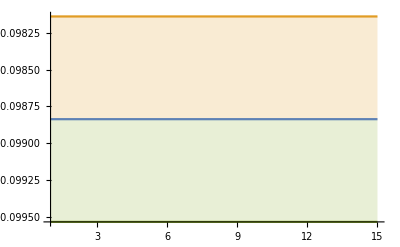

```mathematica
Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,15},Filling->{3->{1},2->{1}}]
```

```mathematica
SpoilHWFLOPlotN3=Show[Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,Length[meanErr2[[5]]]},Filling->{3->{1},2->{1}},PlotRange->{-.2,0}],ListPlot[{Table[{τSteps[[1,i]],meanErr2[[1,i]]},{i,1,Length[meanErr2[[1]]]}],Table[{τSteps[[2,i]],meanErr2[[2,i]]},{i,1,Length[meanErr2[[2]]]}],Table[{τSteps[[3,i]],meanErr2[[3,i]]},{i,1,Length[meanErr2[[3]]]}],Table[{τSteps[[4,i]],meanErr2[[4,i]]},{i,1,Length[meanErr2[[4]]]}],Table[{τSteps[[5,i]],meanErr2[[5,i]]},{i,1,Length[meanErr2[[5]]]}]},PlotRange->{-.03,-0.005},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]],markerlist[[4]],markerlist[[5]]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]},PlotStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau_{\\text{steps}}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3(\\text{NNLO})",Magnification->1.2]]
```

-Graphics-

#### QCD LO - gauss

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={430,430,430,430,430};
NWalkers=200;
Nf4α1LoopBig={0.21556,0.21556,0.21556,0.21556,0.21556};
aList={1,2,3,4,5};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
csvData=Table[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"],{xx,1,Length[aList]}]
```

({mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.02011709666190358, -0.019499723397324843, -0.021026933032086314, -0.020261590678898444, -0.01964212973289341, -0.020788057544307216, -0.019313349464755374, -0.019304072503694928, -0.01935281446386357, -0.020889519293245444, -0.021005015753470538, -0.020773052158405955, -0.018259064841611296, -0.017920207157678704, -0.017142886096823632, -0.017345768391658103, -0.017643654406136362, -0.017593412505047885, -0.016667824101856805, -0.017892981284363414, -0.018216650471426427, -0.016971762717311656, -0.018043831578838824, -0.01850430224345957, -0.017762989620796362, -0.018977397602104443, -0.017094134505530618, -0.014903535232561422, -0.017047256347028212, -0.016921596906645842, -0.016390092058770896, -0.016268082434213238, -0.029871472310502554, -0.019419337624221985, -0.015125660575537877, -0.016833902659089135, -0.01752138392270616, -0.019283148006205942, -0.021521999295476428, -0.02175353503396709, -0.01989990578338093, -0.018062481621339523, -0.024621624824538647, -0.018861540058115512, -0.017377560062914816, -0.01713893889626031, -0.018411370843553477, -0.018108681622385346, -0.017461361666475043, -0.021958571678221458, -0.01905518564105858, -0.017898996096205298, -0.020530488341398964, -0.020867474956224496, -0.018269806875871587, -0.01944549162540826, -0.018918650524749565, -0.02110639440740522, -0.02220449913379573, -0.01854239554539979, -0.01939589663084976, -0.020148642646768727, -0.022316579340348763, -0.02113628359146604, -0.019720498141409373, -0.019266144567371888, -0.01892814077301672, -0.018795431401736652, -0.017003440072827083, -0.018192642411108618, -0.01790846823540348, -0.017741010715926615, -0.019267547628652654, -0.018846521435240154, -0.018590982829453987, -0.018449733350850966, -0.0181649310823322, -0.01940761451063581, -0.01856227521073707, -0.01912778623740177, -0.02689290919764424, -0.020642508677950724, -0.02099097941793675, -0.021609516160383806, -0.02387823845864989, -0.019479895132695903, -0.018768940893793905, -0.021539130330840726, -0.020417719664395154, -0.02072648597565141, -0.020500738902256496, -0.01942651230791555, -0.019276823858890797, -0.017876254544319622, -0.018780616456181624, -0.01834753763038282, -0.019816225496402957, -0.020289898706621404, -0.02136824309611361, -0.020462490148909857, -0.020243545373567314, -0.019817218187135978, -0.021798097326325087, -0.024365410768849467, -0.02383276535754605, -0.024607539201894, -0.024179512140507224, -0.02074578774291171, -0.019589649326070428, -0.01901314492844615, -0.01992226335640102, -0.019888289158832274, -0.02036247458829793, -0.020019468016452567, -0.01958382357592424, -0.0197023182470123, -0.023671772148282904, -0.020588319071603658, -0.02391993227509651, -0.022300503660941374, -0.019044138529794613, -0.02077824517462241, -0.020997137925807607, -0.021457892267327795, -0.021378583591721397, -0.026513889900336783, -0.021853297513111793, -0.021614362194042922, -0.02268944724002825, -0.02174137643638983, -0.020098631729578615, -0.022221095322980715, -0.0199734057966003, -0.020573725073477614, -0.021602106551539806, -0.022067563987076846, -0.024929963168801028, -0.022042591293644366, -0.019821143759801298, -0.020737329469055023, -0.020374615540204005, -0.02412690505115164, -0.02013224151763902, -0.02233711297716485, -0.019038269110032025, -0.01883016125512066, -0.01782274473960436, -0.016353273421159904, -0.017294365771743734, -0.016144921400466944, -0.015920250369782854, -0.015502822935197818, -0.016399013569733462, -0.01508469819919792, -0.017807302070231037, -0.016336643998586302, -0.016812885608031687, -0.017188797190285175, -0.016961328923984574, -0.0169792681920532, -0.016749931116462582, -0.0235092421305217, -0.019467151254806567, -0.018359160369647656, -0.020827724886944576, -0.0215640397120611, -0.020393118043922003, -0.020959868628795016, -0.015735506697901264, -0.01554348055551834, -0.015264660662002511, -0.015548497067565658, -0.014968412861964783, -0.014798593554794412, -0.01617049259934815, -0.01650135588774229, -0.015596698741816418, -0.015374727340333566, -0.015585701924115842, -0.01756188090773501, -0.01714245353944229, -0.015840722052817866, -0.015140245702007896, -0.01478068007066871, -0.015049526664386878, -0.015322743427532749, -0.015765304862940237, -0.015285110060309278, -0.01518879257875295, -0.015644284368894038, -0.016044107630938793, -0.01486647897264017, -0.014647976665487668, -0.014928990867786374, -0.015131786966740314, -0.015373788462645734, -0.016654946394542326, -0.014948061911747704, -0.014051984353151564, -0.013642395489737159, -0.013666757006549563, -0.014248074276099908, -0.014228975000154971, -0.015223445260631916, -0.014566026693722721, -0.015255620551993875, -0.01638772653016585, -0.018640845889861406, -0.019323001673846627, -0.018396553798455548, -0.016861039935830133, -0.019028189190781135, -0.01810362609479542, -0.017363688083017487, -0.018111720419587363, -0.01795151101594817, -0.015693488007600814, -0.017481063271358288, -0.017568630220126724, -0.017606910136240276, -0.028321250659409155, -0.017854222760281938, -0.016103483525364823, -0.017038480679885015, -0.018044074372124835, -0.020327210412693975, -0.02096221340490172, -0.020502465883928504, -0.02029641602011638, -0.019682981184157313, -0.02010016095055732, -0.01788337641840051, -0.017862551800367926, -0.02140329292664719, -0.016908030012528174, -0.018690585493128572, -0.0239198684853217, -0.021942075393915426, -0.019086612465334718, -0.0186894448147645, -0.018778112045597026, -0.02053144032768974, -0.021204621191416723, -0.019605181296697034, -0.01924792136630602, -0.01579453263150353, -0.017282393536286227, -0.017418016392542444, -0.017096746271460232, -0.018968777704096072, -0.019802401727136945, -0.021234695992075597, -0.022738262966125494, -0.020174630032258962, -0.020982679312701615, -0.019597298396007216, -0.023395896567883163, -0.020236195415386217, -0.021622111777034065, -0.019819864825178897, -0.021224033364773673, -0.021337315600065493, -0.019114524753180227, -0.018548589242626576, -0.01746519619208745, -0.0183141971011756, -0.01734631304268152, -0.017756432381689145, -0.018711460001958485, -0.01904380659648159, -0.017920353309769942, -0.017005299814804847, -0.01709926025983921, -0.016765081221422146, -0.015840536586177404, -0.015794313492986867, -0.017409811882621605, -0.016710905137906025, -0.01746120696588806, -0.01797929951900353, -0.017109078411413608, -0.017685249323460953, -0.01789837503849953, -0.017251144848785913, -0.017272153106094014, -0.01682100879772502, -0.01626843067418658, -0.015977941616679175, -0.016507919323359647, -0.01732883569344688, -0.017330802899550548, -0.018579699186013505, -0.02004997012759814, -0.024389822148052777, -0.023057430117265486, -0.022082660881095076, -0.02254434278255716, -0.0233233095918955, -0.02371904046084463, -0.022037887692979118, -0.021894327709633298, -0.02043802493207351, -0.021612718146155726, -0.0280760697527553, -0.02070565586313141, -0.020709865353560016, -0.023203490103716817, -0.019739202573797902, -0.019276864448322936, -0.018038978025592668, -0.018185833170803623, -0.018878286293068522, -0.020908322873081663, -0.021168428865356238, -0.02090593374710637, -0.021628692664364534, -0.022421957225720674, -0.02233724375518479, -0.022358637103729633, -0.023181317578264575, -0.022435384200789738, -0.02417004380827553, -0.02167669126289601, -0.02848421920111034, -0.02182788785376326, -0.020917751819982816, -0.021007639964333347, -0.019409177530356647, -0.021477268474059362, -0.02639624504422915, -0.022620433325553413, -0.02213341041521861, -0.020116113934001707, -0.02071881792721664, -0.022221888295335758, -0.021943105584489923, -0.020243111463009687, -0.019335478663742692, -0.0206797857555459, -0.02201125994875223, -0.021111852995868634, -0.02068080230131935, -0.01922561598914872, -0.01965824502094565, -0.01983676411391758, -0.018673531027308867, -0.01798400757620132, -0.019047290179987967, -0.020160161535836493, -0.021805189311490506, -0.020343251020419836, -0.019970360379771016, -0.020290548896587466, -0.021164373509508536, -0.02165511641653742, -0.020671791959111167, -0.02127761963897215, -0.022503117013581295, -0.019997464946657818, -0.022972770427324093, -0.02174978285054435, -0.02070371003994728, -0.020464062952669344, -0.0202906918152147, -0.020258811915934073, -0.020099052407684018, -0.01960692815176724, -0.01896167988411724, -0.018995300092596153, -0.020476476278406305, -0.020498573245366754, -0.02254643363795386, -0.022976394740703135, -0.023893271959502232, -0.025951150590288356, -0.02703592598433748, -0.03087716315102157, -0.02978244610662241, -0.04031314944662111, -0.03857167404913467, -0.031270427992915885, -0.03484604168732352, -0.03403653775487701, -0.03317758549844596, -0.0395777191294271, -0.03548193983892229, -0.031065215905122564],[0.0022276742387067473, 0.0021540096992121354, 0.002810007372281038, 0.0023329611588107212, 0.002417751713609959, 0.0038393065107641226, 0.002744192557362726, 0.002315861117559058, 0.0021743533506798115, 0.002808004178714711, 0.002811435363061937, 0.0025663241000195686, 0.001865277019502008, 0.0018628908545449674, 0.0017821956655485465, 0.0017789852729625862, 0.0018746243859819928, 0.0019003444498438323, 0.0015977404331026237, 0.0018992656910319765, 0.00203370280705888, 0.0017756283845658098, 0.0018408281427283555, 0.0026092948841739774, 0.002066186823697894, 0.002620464056853636, 0.0021321466531736546, 0.001574117498194425, 0.0023874116467699083, 0.002244534648304576, 0.0018183985939204362, 0.001872510655104816, 0.015035722125707418, 0.005631825976773929, 0.001749391528721191, 0.00237781578801694, 0.002081448935501896, 0.002696971566744901, 0.004463836997133589, 0.003712047587746967, 0.0030588560246669547, 0.002162088477308239, 0.006721255289709618, 0.0023750659970934312, 0.001885476522903283, 0.0017936142101204764, 0.0029268730627181124, 0.0022329401192275927, 0.0023362784067022294, 0.004839291406825235, 0.003152462963117696, 0.003071035661716445, 0.004650778595774879, 0.004857003837689258, 0.0022477695873377042, 0.002815722156198501, 0.0023715917276699093, 0.0031310285988502256, 0.004424013134784878, 0.0019242415635919521, 0.0021458643483276796, 0.002238391589059189, 0.002956237549369018, 0.0025995464550790702, 0.002078719121903168, 0.002033502446085311, 0.0021276370348978207, 0.00227969861324577, 0.0021668870167678464, 0.0024137874810383365, 0.0024342199311222514, 0.002280691456430101, 0.0026957923418113993, 0.002766445151311108, 0.0025549776890396725, 0.0024300266641640272, 0.0023809197236805946, 0.0024903306139940086, 0.002484119433087847, 0.002665381184533886, 0.008009136307259988, 0.0025873276004841302, 0.002773413694162396, 0.0028239145919287012, 0.0046961742485097, 0.0025373305792503135, 0.002148661080712875, 0.004333336265970017, 0.0028481234799388835, 0.003143402455484145, 0.003032949846701874, 0.0023792346330504133, 0.0022376443932483306, 0.0018858555677316972, 0.0020594086403964225, 0.0021692600160950364, 0.0028117677823683808, 0.0027044289883713956, 0.002979196439377887, 0.002565428503651395, 0.0025064847930611495, 0.0022857430266600264, 0.0027099192038162467, 0.004452540200975224, 0.0032291103515605124, 0.0030955327672776392, 0.003110863117198103, 0.0022343978354269767, 0.0019548896271986433, 0.0017869966205675356, 0.0020048266420949886, 0.002334146745071866, 0.002644744169627836, 0.0024897468993458306, 0.0023243266255085185, 0.002344564414870596, 0.004880009822622654, 0.0027202563300291424, 0.005066413646432492, 0.0035418042526193074, 0.002887983090302913, 0.00396170113821419, 0.0032721299191510234, 0.0033350002209279386, 0.003312009135505786, 0.007015897879246285, 0.003643945369003622, 0.0034228178910267, 0.003658962473631619, 0.0036596348113421325, 0.002981779204710444, 0.0032679573905320643, 0.0027423451031026494, 0.0029013372587480407, 0.0032282330279440595, 0.0033302403062613647, 0.0038902952609612637, 0.0030810666898953747, 0.0024166155111541646, 0.0025679805288677505, 0.002750730004626997, 0.005575233971729069, 0.0023781400740623183, 0.004017929180831116, 0.0024489990159068894, 0.0028858918347800617, 0.00259540420193851, 0.002167562646634592, 0.0028958815495548156, 0.002080143042915984, 0.002128021999846133, 0.001904760178846341, 0.0025090462442613985, 0.0020903509290485533, 0.0027571009641767764, 0.002247577536170296, 0.002301146315885887, 0.00244261476915933, 0.0021634257857695376, 0.0022944915297516675, 0.0022480138089275704, 0.007163080713697285, 0.00356660756518343, 0.0032370607061460717, 0.005446138138625898, 0.005790397947385099, 0.005440065997885463, 0.006113745651203277, 0.002284466330103896, 0.002252711739689598, 0.0017624283711375713, 0.001797668338890659, 0.0016974141736584994, 0.001813057719920151, 0.002122200527235589, 0.0024129854166096702, 0.002082771663569293, 0.002015879497010402, 0.0019245197716276758, 0.002443169699361404, 0.002314520660008849, 0.0018184992279927747, 0.0018652337153951778, 0.0019948768796540168, 0.002130370162816543, 0.0020145740154768666, 0.0018833583424893309, 0.001974267678914254, 0.0018412234146596997, 0.0018680175991180501, 0.0021219715876090854, 0.0017710698964270909, 0.0018482245983108753, 0.0019029803301811336, 0.0019026373861276446, 0.00205190653887729, 0.0027277801561675632, 0.0019891323485003005, 0.0016661034742890958, 0.0017260502260875896, 0.0017474881062374552, 0.0017646657269446244, 0.0018143969041463483, 0.0018991179236947048, 0.0016881289658468072, 0.001743617830744683, 0.0020732301940218287, 0.0025796746635346176, 0.003193871811799802, 0.0026860206712946626, 0.0019915071746290456, 0.002932445837840472, 0.0029383618839551712, 0.0024634714655324156, 0.003323709571522843, 0.0034588112609720213, 0.002442412398243892, 0.0041698437994137786, 0.003981495209621165, 0.003394960732877747, 0.01320394735252378, 0.0031462571474163625, 0.002319011110572248, 0.0022776172646012446, 0.0025686322532071774, 0.0038383295455353436, 0.0036387911651732242, 0.0037681521874839766, 0.0037470455653098632, 0.0032780156548513025, 0.003869780740439265, 0.0027565821498951185, 0.0034477997418246153, 0.006563279061632398, 0.002964346593532792, 0.003637079376875008, 0.006639752228722916, 0.004741970927527005, 0.0030195839365124216, 0.0036641165266794906, 0.0037036680789595687, 0.004371384886867563, 0.004197298551667392, 0.003212091466672636, 0.0034604499694992595, 0.002053584595381232, 0.0023978176942677024, 0.0024387321538657976, 0.0025188554987875447, 0.0027918144426268402, 0.0031054418386044285, 0.0033181525385007514, 0.00354968087562312, 0.00314750768739786, 0.00360426142575763, 0.0026679777348180386, 0.004028074827243635, 0.002882151923348439, 0.004020083826537639, 0.002630480208018152, 0.003075621378797405, 0.003515079462017656, 0.0026033365394277246, 0.0022610581702204816, 0.00229649760222586, 0.002432009357947266, 0.0020931714197150826, 0.0022358213652349935, 0.002252970288381492, 0.0027790964262875343, 0.0024274985678230418, 0.0023130680349045976, 0.0024105876739679197, 0.002481733533422368, 0.0023346176427272644, 0.002007518545295302, 0.002426027132653715, 0.002182484956997314, 0.0022706195855210515, 0.0027435126097465727, 0.0024279366451287606, 0.002801839795652488, 0.0025701648393097356, 0.0022935320950176127, 0.0022151628995939906, 0.0022054531381002496, 0.0021126372941758257, 0.0021329446063788103, 0.002034938195295663, 0.0021144656432643253, 0.0020944384198302215, 0.0023601555741904856, 0.0028541397878011614, 0.005395702046342637, 0.0036055023037352457, 0.002687824069802856, 0.0026506785697640593, 0.002883885002697738, 0.003078762260939706, 0.0025821724574736516, 0.0026036748000231196, 0.0024015678684155333, 0.0031182784105105573, 0.009656931818686591, 0.0029037262839939695, 0.0029813889373175376, 0.005549794913732205, 0.002748221042392488, 0.0024615265918450386, 0.0022584608217270053, 0.0022203978387496056, 0.002324989570218344, 0.002440016759627957, 0.00260989283032959, 0.002452026886098355, 0.0025284248037694868, 0.0025510461654611512, 0.002548393187149144, 0.002579772951484689, 0.002766381895528037, 0.0027301298819811973, 0.003286900727759903, 0.00277048592619997, 0.007104171079938982, 0.0035050390032940514, 0.00292339413550358, 0.0030461495232149156, 0.0028499571413415823, 0.0034256514857419545, 0.0046227002992448914, 0.003793115740085343, 0.004213167016473549, 0.0035658405311474136, 0.003601423839308463, 0.004428946042802336, 0.00445356690613774, 0.003756116378260414, 0.003573833159934593, 0.0037002381623756743, 0.003663468689383948, 0.0035454666275537587, 0.003571614611313617, 0.003388119483740028, 0.0035321329276855936, 0.003545990358242752, 0.003615383797736261, 0.003508532228930455, 0.0033500287979337548, 0.0034672206496715293, 0.004034307969058282, 0.0037271994973714926, 0.003678203650385044, 0.004099294679197239, 0.004827508735080097, 0.005382777401378318, 0.00527056471654458, 0.00495019001257078, 0.004987904839909833, 0.004697197544413755, 0.005852689670817642, 0.005014259617143073, 0.004640935337693675, 0.004738224627205422, 0.004839478091611486, 0.004964127602381253, 0.004678147283987541, 0.004649471453859951, 0.005091688386617921, 0.0049385229344977005, 0.005370919402048544, 0.005286631804220267, 0.005220587493210837, 0.005069180791999692, 0.005056623712049735, 0.0054107071296761065, 0.006019760263017891, 0.008237504236585444, 0.006396810877323217, 0.014904359592980369, 0.009420956463482797, 0.007100708290341149, 0.010366075531132007, 0.007731448914196828, 0.008534966266293787, 0.012124149442269123, 0.010360713776823427, 0.008011607054666347],-0.0169233,0.000414197,0.484657}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.016504581801258324, -0.016928080672936264, -0.016789726031537573, -0.017365784429360633, -0.016914891224542667, -0.016367230515301624, -0.015895059078124198, -0.016005189116913256, -0.016176838348769165, -0.016276604904645463, -0.01644793575633194, -0.01630543445553642, -0.01674188372838467, -0.01723577463727057, -0.016578565554714014, -0.016387279982738843, -0.01672597555015667, -0.016735106355114614, -0.016651826151360804, -0.016755644752535367, -0.016633901947600817, -0.01669552547218583, -0.016481795053688627, -0.016902268609702356, -0.016897764617249948, -0.01720386017965387, -0.017546006559214074, -0.019459606077830316, -0.02426834474684534, -0.019272929292570382, -0.019117779765265352, -0.018359240593602416, -0.01792167973899825, -0.018424336212005135, -0.017694784557864055, -0.01730512618703303, -0.016939598039374386, -0.017128143216001767, -0.01694178012747108, -0.01667463556385533, -0.0166226770448734, -0.01704060930551052, -0.017489320701293498, -0.018031179308625717, -0.01748058239733811, -0.01776204177175652, -0.017562123456109455, -0.017401830104071755, -0.01800083729467762, -0.019431717112025695, -0.01760355492678689, -0.01791143959633227, -0.01902594893905232, -0.01831628012310882, -0.01821110492414555, -0.017381158479360448, -0.017227258214754463, -0.017805012859496823, -0.01793179168961955, -0.017530761677078854, -0.017604835498396344, -0.017958566164880462, -0.018022307728160904, -0.019169424518102267, -0.019001532437244825, -0.018785515968355808, -0.018728401766308092, -0.01916757348326475, -0.01913223395135464, -0.019787487359860894, -0.018961373467249982, -0.018939152532565624, -0.018252423663597504, -0.018687743201616768, -0.01854178967904052, -0.01846755804191648, -0.019388501545817168, -0.019268337244710106, -0.023004868182096325, -0.02093185594496948, -0.019464508847332196, -0.01985575107808767, -0.01883506578195197, -0.022668259070288924, -0.033861660822438674, -0.025522415326894893, -0.020529118581782177, -0.018940026450030508, -0.01933148359420685, -0.019933829194466787, -0.01919920621089815, -0.018770428986948598, -0.01893257748813185, -0.019121483893079272, -0.02161518081189176, -0.022620067394301654, -0.024771311034341863, -0.02158214734294915, -0.021318720402678185, -0.020314938106110233, -0.019408296153646185, -0.020635845086714913, -0.020665521320529887, -0.01848416521401509, -0.018550942966877478, -0.02090507244003948, -0.019616980841741793, -0.019260567591291952, -0.01938828372518431, -0.01823947723361075, -0.018491009399273152, -0.018548234408402486, -0.01863442249336952, -0.018840026780504802, -0.01808985802203882, -0.017355547939352275, -0.017416009229020465, -0.01728972118331073, -0.017224088718305608, -0.017655970770707626, -0.017314108005083394, -0.017839564716782476, -0.0175289182233233, -0.017538459628896566, -0.01770716667405515, -0.018073369037725145, -0.017897177883069097, -0.018410993170949633, -0.018856986014771815, -0.01925310488897314, -0.018301328773707812, -0.01837018310106439, -0.01936619439735266, -0.018652171755765317, -0.018062744529420038, -0.017944266209709077, -0.017639619366052673, -0.017844527395303792, -0.017617822918056913, -0.017318527339135928, -0.018446289883846324, -0.018362980746338922, -0.01914291234419643, -0.02163483526933009, -0.02134485537745635, -0.019051747369296473, -0.018278771577417495, -0.02174496781049716, -0.02031309396944717, -0.024074386164725972, -0.0233126668787765, -0.019655410685872687, -0.01856227539019787, -0.0176957744809977, -0.018785633089985296, -0.019533061029304678, -0.019319381392285482, -0.01865331897468559, -0.018576584201602887, -0.018700793775867537, -0.01889133241700161, -0.019062264636661795, -0.021022020581832754, -0.019310235628105746, -0.021222768511506545, -0.01902896855760962, -0.01850950107414803, -0.017903649863486464, -0.017545800556915004, -0.016750670888076018, -0.017278566972554275, -0.016453443340266702, -0.016886250913454005, -0.016553046737085114, -0.016343925810661408, -0.015617328122436446, -0.015943246343039733, -0.016253171431787953, -0.016441654077018305, -0.01631689182393718, -0.01620494852083756, -0.01595642619570366, -0.016145414946097482, -0.01580128576058373, -0.01585230842940459, -0.016108915782523096, -0.016313703684731645, -0.01593676844300474, -0.016024479540033276, -0.016233625888122688, -0.01645720376619245, -0.01669250298414712, -0.016731803613148546, -0.016759321951008887, -0.016524262901090023, -0.016607230269314075, -0.016697271512453444, -0.01687776854129146, -0.017223438378728438, -0.017981962815784472, -0.017091508716138085, -0.01716124160398827, -0.01691930575379928, -0.017482254645630822, -0.01726838971891335, -0.01784842945895114, -0.019290445594544965, -0.019016468744311586, -0.01876471515925794, -0.018677246501370908, -0.01973538875205458, -0.018889940538032987, -0.018824521568318514, -0.01810638555531727, -0.018159109972491982, -0.01818017004095946, -0.018548239971526704, -0.018932533046488568, -0.018554686025440574, -0.018691774541565166, -0.018035260168856537, -0.018028426394768943, -0.01766801626687666, -0.017855273002993353, -0.017648770101027243, -0.018178926147625226, -0.01843506816503019, -0.01818327756707908, -0.018470029326126618, -0.01858710095718173, -0.018655653201505307, -0.01855896605813217, -0.01813214231649395, -0.01815967554142061, -0.017382510778625206, -0.018449919094095196, -0.01879665368371365, -0.01868886573060032, -0.020338675666778844, -0.021324629596338268, -0.020063713225108047, -0.020005534113116546, -0.019794380854421808, -0.02054024088198972, -0.020144284057457523, -0.02094003968794837, -0.02094707865587161, -0.019769116870998277, -0.021938825005157026, -0.024242195687570554, -0.02643859509402852, -0.030548897946508606, -0.028519243966501972, -0.024533442363273813, -0.02326829985522048, -0.028510591147702213, -0.031100331101814812, -0.028010923686155046, -0.026644993727110534, -0.024549495182070155, -0.026862903274063956, -0.026964974904047652, -0.02460352229125623, -0.02454474625848967, -0.023939960735443466, -0.026586754150804644, -0.023634554107985695, -0.02427649914058465, -0.025425547039273747, -0.025226922182626562, -0.026840054038054388, -0.02725370790839001, -0.025618600015198827, -0.02614695418338671, -0.025896301439275054, -0.022208383981125557, -0.02066716954445658, -0.020861866586851067, -0.023133939936036754, -0.02059406132518493, -0.023999808247076097, -0.020174402924353248, -0.01983446610101405, -0.019148421752496682, -0.018552304160419548, -0.01947386361776877, -0.019404559341925982, -0.017694514703196117, -0.017801858230015805, -0.018269336150428254, -0.018639851054146138, -0.019466146597795952, -0.019833686653829546, -0.019649869623940018, -0.018720135926693336, -0.019972428935605475, -0.019441715868722162, -0.02013241831504563, -0.020210717048568468, -0.02154377289230107, -0.021093076959859087, -0.022718905947560004, -0.022566594317675458, -0.022974603772885443, -0.022371991356925188, -0.022561773879919957, -0.02167350807076854, -0.021200384900956562, -0.02153647606623842, -0.022827781080172374, -0.024289665699556737, -0.024056610336381477, -0.026061675700714913, -0.028301042617316564, -0.025405556467855854, -0.02340740832019951, -0.022902806543034233, -0.02541184626388829, -0.024332164113406392, -0.024144043028342638, -0.025059769017800246, -0.024171887986041446, -0.025473623712677345, -0.025655545098472145, -0.023037242237408502, -0.023769792314479943, -0.0225483139162778, -0.021430882813608623, -0.02141585168679245, -0.02135840999451389, -0.020367182744268346, -0.02033484548146653, -0.02078392316529874, -0.021609798594025672, -0.022542700523425722, -0.026205364778080574, -0.02361338609498745, -0.021760245237579526, -0.02030606722897416, -0.02053508856589659, -0.020418626564015135, -0.023008910328459135, -0.023234716640774897, -0.024094574330259473, -0.0279840654659207, -0.023014192884315346, -0.022909869707052895, -0.021337600367348268, -0.020481607217559938, -0.019314008393186723, -0.01895021798526369, -0.01860739811767818, -0.017769700074869135, -0.01665154825927428, -0.018062003313829646, -0.018358750573799223, -0.01802117273836337, -0.017921823345014905, -0.018937972050930625, -0.017444468982166728, -0.01738722436881391, -0.017906790975921096, -0.018758284489827182, -0.017255371560085917, -0.016426875200585767, -0.016850590453665992, -0.01610134980910803, -0.015854582293114938, -0.01582801808576135, -0.01595032474934427, -0.01564785316728138, -0.015585511610978799, -0.016284718466432483, -0.016105634962819058, -0.015995960719094413, -0.015965919166088433, -0.015568501195498697, -0.016040639378232854, -0.015313417814834196, -0.01567883550534531, -0.015653276708878883, -0.015097965763034765, -0.01509768621118174, -0.01500881548196291, -0.014909984850747285, -0.014866855660515344, -0.015268148721000142],[0.0011208294748743211, 0.0013268531910972734, 0.0012452204958284887, 0.0015923094922982118, 0.0012537569061683196, 0.0010128672869331838, 0.0008596692515961891, 0.0008578592650474232, 0.0009168578260591187, 0.0009390163577727186, 0.0010614619815701451, 0.000996144799022432, 0.0011689203294946806, 0.0015639022288098194, 0.001278122621810824, 0.0012071282420972468, 0.0015167123783993597, 0.0013264850778037993, 0.0013155761027746162, 0.0012618948905085599, 0.0011556883859341976, 0.0012274473413748188, 0.0012004516396932796, 0.0013540718873264728, 0.001240172431481092, 0.0014049716196299496, 0.0014672328954086805, 0.002997053152413754, 0.007950791061616998, 0.0029001164427419628, 0.0021115372763480847, 0.0017317612026886814, 0.0015388870920988538, 0.0018141485057701443, 0.001373775740286268, 0.001199965277496449, 0.0011870632595274101, 0.0011094144753963763, 0.0010337396061011952, 0.0009021843244719789, 0.0008692849104852363, 0.0010556176847846927, 0.00115466020249856, 0.0016487088098611552, 0.001226608898480321, 0.0012961462462479667, 0.0011953682321491786, 0.0012283090689712514, 0.0016017383253103072, 0.00275808303536369, 0.0012272811301858907, 0.0014656727072761288, 0.0024012487082642866, 0.0014710339436725557, 0.0014186746500964669, 0.0011917327475957095, 0.001165497052420926, 0.0014254972507310498, 0.0015369576835449178, 0.0012240161996914087, 0.0011817312154933292, 0.0012853841174264703, 0.0013835395130978548, 0.002113759522512355, 0.0019025472073943075, 0.0016787346580636631, 0.0015346738619266376, 0.0015279772722409531, 0.0015730151115149688, 0.002055372272532933, 0.001623755630958649, 0.001663686743774481, 0.0013837969943882335, 0.0015600743783707406, 0.0017041605465379895, 0.0016406251137768531, 0.002122697614089226, 0.002061829547985046, 0.004925242803171667, 0.003409075204442081, 0.0023163505652458206, 0.0025679516174717883, 0.002075919467457242, 0.005279740797828619, 0.015812897527630904, 0.007733754977355738, 0.0036148582012188973, 0.0019183262882886834, 0.0019518834907877344, 0.0023019689111152177, 0.0018579321506070239, 0.00163953011553242, 0.001783793889590694, 0.0017357208879898983, 0.00335521531562981, 0.004094097477725539, 0.006461465295456, 0.0030130561315951368, 0.0029392410465419704, 0.0024134804828365906, 0.0022341003722756063, 0.0029479745086910215, 0.0032787434724437644, 0.0017679545681236319, 0.0019059593132388368, 0.003846232397493531, 0.0029681961769232644, 0.0028694429628738196, 0.0026073812478140243, 0.0017784951824737203, 0.0018749355113798854, 0.0018194359852712937, 0.0018770221015998617, 0.0018783333236512165, 0.0014845750700428087, 0.0012066148467652325, 0.0011320324199582453, 0.0010593974717571536, 0.0011128159946351395, 0.0012930305224541866, 0.0011438327664256218, 0.001358809968031029, 0.0012373515235034676, 0.0010892278121099523, 0.0010955203984525073, 0.001175169864300583, 0.001123934441324611, 0.001256521629447684, 0.0013936392517173146, 0.0016664074045781101, 0.0012236134684029964, 0.0012242036545133208, 0.0017832373854252909, 0.0012711734627466208, 0.001132704464531373, 0.0011069537681071163, 0.0010151539427054527, 0.0011081124407527714, 0.0010827437104688525, 0.001031490664242244, 0.0017222103252684557, 0.001621873797213919, 0.0022377450169858235, 0.004606767247271896, 0.004005732704185594, 0.0020742539347706635, 0.0017447924011510102, 0.00517872175726193, 0.003893242306817007, 0.007221752596515372, 0.006293220916695754, 0.002945347950471154, 0.0022271916175523386, 0.0015804426449812507, 0.0023967709519317434, 0.002914429960836546, 0.002373075582789153, 0.0019139552444466094, 0.0018392727504046055, 0.0019647341907430738, 0.0022168324194363023, 0.0026610537574425445, 0.004561272728702923, 0.0032593229140463822, 0.004876978696399822, 0.0028166052075089304, 0.0024594599718972625, 0.0017583094846332782, 0.0014887817273194527, 0.0010469926288375873, 0.001637869480407181, 0.0011049332851883224, 0.0012604139185235267, 0.0009957842450034223, 0.0009079136378586526, 0.0007719445644952179, 0.0009433753908705769, 0.0010498921199657127, 0.001073623965051462, 0.000998950782655587, 0.0009545430549677079, 0.0009042260400058018, 0.0009128884545579201, 0.0008052548428559671, 0.000850057854287797, 0.0009381678079677257, 0.0010844330525177776, 0.0009566965328324728, 0.0010645941526839211, 0.0011485945329338422, 0.0012403844973400333, 0.0012224137778590514, 0.0011911341476787487, 0.0013281695036785324, 0.0012776749195017052, 0.0012504857136354413, 0.0012899088160792623, 0.001550660978271341, 0.0015939553019224952, 0.0021896118617889117, 0.0015623106257702066, 0.0014428668315447102, 0.0011372283263692863, 0.0013910225735288399, 0.0012713284598970384, 0.0014644973313657171, 0.0020536682887711787, 0.001896675984037165, 0.0017868608737241208, 0.0018325985056867724, 0.002487124189907661, 0.0020339918356264697, 0.0020868969501106702, 0.0016560002335375382, 0.0016084658232474146, 0.001534142766054077, 0.0016696610080886467, 0.0018777467334981737, 0.0016340747922491026, 0.0017364304614574232, 0.001405315956457157, 0.0014761465086400886, 0.0013194853343863214, 0.0014708022085186054, 0.0013669659360965125, 0.0014258222858207755, 0.001586498907356034, 0.001512811457347776, 0.0015239471946999477, 0.0016223208342238706, 0.0015538618381052028, 0.0014610052330341111, 0.0013180207084388257, 0.0013800464865146012, 0.0011315288752820007, 0.001509615863001798, 0.0018096761037590353, 0.0017523965759718852, 0.0022336169082168766, 0.0027872729032720135, 0.0022442078366835894, 0.002176514216556717, 0.0022467990754841084, 0.002721950282275581, 0.0025268086645782676, 0.0034497945669217447, 0.0027220134790742635, 0.0020684319916734538, 0.0032263140166600224, 0.004340315433581399, 0.005322751685379636, 0.0070324733204464055, 0.005987048424942781, 0.004307929765899818, 0.00351023729864597, 0.006118744987772638, 0.007460304622981041, 0.005983397642969017, 0.00519610268259713, 0.00429094949646105, 0.005297617945517283, 0.005184200453570499, 0.0037109710779840667, 0.004194989364470784, 0.004255189153082485, 0.006028419156110784, 0.0035790245739974846, 0.003591525556914059, 0.003909464432699101, 0.0039133481755739274, 0.005065386444910682, 0.005212812347151113, 0.00490145303272515, 0.005282895898649117, 0.005654221594269379, 0.003259017989349629, 0.0024339077602283615, 0.002646424778484558, 0.004163967691790908, 0.0025558167721063236, 0.005303706435000099, 0.0024790893415270595, 0.0023659986652950116, 0.0019685498511889886, 0.0019206303747458283, 0.002630000144238034, 0.002343356774122106, 0.001576798108600539, 0.0016886175018474535, 0.0020326413545722843, 0.0022573343452765428, 0.002617878612497237, 0.0027226324742002307, 0.002398737944292912, 0.002085923432577777, 0.002741019060544281, 0.0023099816578913477, 0.0026531803841673154, 0.002630930965612778, 0.003295153025628985, 0.0028186213239351668, 0.004399854121291993, 0.004122664268319926, 0.004641265527204992, 0.003915889669666325, 0.003467303304031339, 0.0027197858054035604, 0.0026861337517666084, 0.0027343613470396503, 0.0035794403505545335, 0.004578305843128428, 0.00458861822738914, 0.0060942228175863, 0.008044072789279093, 0.006035111347476411, 0.004117601905051098, 0.004244778954621863, 0.005278804569266557, 0.004826976067981614, 0.00414989759955618, 0.0044237344227367114, 0.003855387097696324, 0.004733026162817063, 0.005230784915507147, 0.003656193605297222, 0.004060063059541378, 0.0035000294731978273, 0.0030127800793913586, 0.0028708210694883564, 0.002582557718149509, 0.0025055336601405654, 0.0024560299135212545, 0.0024983886502132646, 0.003192535354102055, 0.004578805937874479, 0.007786396685143219, 0.005578730198942845, 0.00403239257034304, 0.0026874145816308337, 0.0032302999707802707, 0.0029759616643528857, 0.005530296949929873, 0.005866297420675632, 0.0063051579533577205, 0.009726103592311134, 0.00592590699560799, 0.006096905096947109, 0.0051229865262176644, 0.00433811985593681, 0.003213725910123336, 0.0027758328304391434, 0.0028584708918492773, 0.0023672066729933075, 0.0015648092833174308, 0.0027798437746560465, 0.002826409907633552, 0.0024831105460326164, 0.0022012974647223527, 0.0030348819732580593, 0.0020128441411643434, 0.00212364023186319, 0.002373568860261621, 0.0026062816026956068, 0.0015783388576425899, 0.0011676894378138806, 0.0013302519440299406, 0.0010925218650324458, 0.000980728403623252, 0.0010672274056494834, 0.0012832503370442162, 0.001127859760733885, 0.0010031180634831448, 0.0012293229222200125, 0.0011869827648676929, 0.0010456083232294384, 0.001161045483617393, 0.0009479172350778642, 0.0011767775996306701, 0.0008822822251949488, 0.001082589168585718, 0.0010795358922078878, 0.0009434751206069595, 0.0008708467048715305, 0.0008300576241189549, 0.000858091983492772, 0.0008152573544724891, 0.0009450103829742674],-0.0146444,0.00026626,0.182419}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.012480825137815644, -0.012483949910193165, -0.012471547013687103, -0.012725138374391612, -0.012887005841057703, -0.013221201328626286, -0.014646426661141828, -0.013440038328808083, -0.015213216732081133, -0.02443702885765399, -0.014136991779921216, -0.01407106583125551, -0.01391931873681302, -0.013983276267356366, -0.013250870037613854, -0.013607323862129286, -0.013886235192950283, -0.014306698931248673, -0.01450508405612043, -0.015563850595328676, -0.01623734986388417, -0.01582309710360624, -0.015495294883193827, -0.0142390751790428, -0.014406725690053274, -0.014534352938595235, -0.014133813962183312, -0.013936009067295476, -0.014339610385951183, -0.014462083197191718, -0.014375139932395382, -0.014581993788306408, -0.014767145218359293, -0.014465781614880822, -0.014819309654412874, -0.014996055113474717, -0.015018797125311692, -0.015163071775948108, -0.016232318425630585, -0.015739325859259794, -0.016028672302226914, -0.01631873842204117, -0.016165330894121296, -0.017112624720700166, -0.01984337346413561, -0.016006175462027327, -0.016657354787991775, -0.017290613956423114, -0.016832871592111675, -0.017243105929482038, -0.019405990793875935, -0.017797089077138083, -0.01761983011458466, -0.016618500941415336, -0.016986102634892523, -0.02623349091537921, -0.01951450989316671, -0.017380408535800407, -0.017212223325220335, -0.016618780358267544, -0.016589730857495058, -0.016347973402031275, -0.015465634505950896, -0.015214286807258262, -0.015230207229470605, -0.015329512033201272, -0.01525755237056819, -0.015845041304274866, -0.01550881202496765, -0.015469582998044552, -0.015321311198212492, -0.014752060298820733, -0.014834571624738824, -0.014983690403504783, -0.01467312713319104, -0.014580097033742237, -0.014349005993979314, -0.014483397382996813, -0.014377816016197151, -0.014788643371086981, -0.014824681068255071, -0.014392824157696585, -0.01436832631460506, -0.014413920758023521, -0.014904149076908516, -0.014920625905802362, -0.014616864958103229, -0.014963840131557642, -0.015143334328154102, -0.015858095762045176, -0.01614890259056459, -0.015766002171628997, -0.0161568504762999, -0.01575940165433879, -0.015267978132833808, -0.015336005072055556, -0.01612741322804665, -0.016536461812159835, -0.016524789770254792, -0.016415004398836586, -0.01672315572034959, -0.01698970494542469, -0.016700630692741036, -0.01708680494171629, -0.016721980980999047, -0.016664007238990707, -0.01701228595683595, -0.016935174014347826, -0.01683142693238234, -0.01646547582197234, -0.015796303546991994, -0.015575062317536872, -0.01565456712870389, -0.015695499372089618, -0.015866267601905498, -0.015843523098018363, -0.016074331024015585, -0.01669834135414675, -0.016513924460256315, -0.01645553892948301, -0.01675982276619073, -0.01605661576052252, -0.01578583931594919, -0.01650967014742691, -0.016772675963590944, -0.017125732833227377, -0.016943043297382433, -0.017029102060585874, -0.01663865040816034, -0.017172970856512967, -0.017000423277037643, -0.01717729267056933, -0.018112131285877152, -0.017806106328297683, -0.016504486151557942, -0.015832551130686403, -0.015932447103511504, -0.016905791210487672, -0.017299588312170676, -0.022853123283127694, -0.020116780420316453, -0.020309684536461158, -0.018766484638438892, -0.018756056923853095, -0.02008740530813545, -0.018699148924839676, -0.017208167941928854, -0.01696775529360543, -0.01703516845144371, -0.0168005519534942, -0.017190515732698437, -0.017636495378561746, -0.01708362288144037, -0.016914814317417697, -0.016647933375649702, -0.01673548381727105, -0.01739631582085075, -0.017274124601400376, -0.017642523203872433, -0.017795892325282225, -0.017909708642058726, -0.018180332351340308, -0.017110657342077548, -0.017309328425241088, -0.016976189744232588, -0.016203134962859314, -0.016426112225285717, -0.017065122304523263, -0.01801434734703075, -0.017129389144602946, -0.016794752513864124, -0.016680155561150732, -0.01734346068551593, -0.016514041364272963, -0.016710662125237072, -0.016156485503190522, -0.01659211357215006, -0.01682961670923687, -0.01625388847352468, -0.016411425808187875, -0.01621013477486562, -0.015506200282896062, -0.015824710389625882, -0.016249452251202445, -0.016404631886054642, -0.016430739099868197, -0.016090317108961857, -0.016319921002399047, -0.016270883834978107, -0.017508486318073804, -0.02112855853307632, -0.020480066384558182, -0.01797290913917572, -0.018651060117127312, -0.01689463216382793, -0.015472066588997233, -0.015250650781945147, -0.015013325210105663, -0.014917644174004473, -0.015159213133059886, -0.014919437096294669, -0.014627334233902344, -0.014488064374502478, -0.01441448073106119, -0.014270862600990726, -0.014224649057303354, -0.014237570649405704, -0.014000420635055438, -0.013956332722692744, -0.01410036064572573, -0.014106490559545186, -0.013987898412658536, -0.013838535064514887, -0.013835785054412702, -0.013872762026356435, -0.014028222508360957, -0.014129255052142874, -0.014039540549734712, -0.014071111514619882, -0.014251682118745026, -0.014208703347855133, -0.01408015446504555, -0.014087998885868014, -0.014234734309645738, -0.014020161392441678, -0.014177992699341793, -0.014613340005497015, -0.014617785493420507, -0.014663973149523475, -0.014730056228188461, -0.014594971607825427, -0.014748795761213915, -0.0143648419621239, -0.01440360654397149, -0.014329533046956716, -0.014296440459850963, -0.013993540323011047, -0.014163959015345493, -0.014320791978811184, -0.014372118108286504, -0.014317775285345075, -0.014267097563273, -0.014368703515912906, -0.014420862046626931, -0.014146110734006765, -0.014177321356988713, -0.014005803699204778, -0.014054077353164676, -0.013989106839166305, -0.01394676261880549, -0.014025013371276866, -0.01408983383808672, -0.014044025149057383, -0.014303599756114907, -0.01456146676428146, -0.0149154509842789, -0.01528558396217914, -0.015398235683625895, -0.015457858139337033, -0.014932669515160953, -0.015180381465397111, -0.015469720424781052, -0.01582694622081479, -0.015395296577692773, -0.015426864655314346, -0.01566753864186018, -0.01556581942364929, -0.015228556049796015, -0.015217441928359573, -0.015487544315603835, -0.01577222736862846, -0.015779070643232515, -0.015820896540338313, -0.01578875706514092, -0.015541994486185082, -0.01553732221705213, -0.01584101945541538, -0.015740205679158757, -0.015781810571321175, -0.015032014072256338, -0.015265697001664667, -0.015157783352421557, -0.015126619170167903, -0.015147526896950217, -0.014662173013213231, -0.014524525936559382, -0.01449319662516613, -0.014194533899200414, -0.01390412978296037, -0.0138788486796655, -0.01392880055416946, -0.014280358080731295, -0.014163035304704636, -0.014251231908093468, -0.01394119410454663, -0.014308016298125031, -0.014550581313011426, -0.01501004634184276, -0.01480270919010647, -0.014746608649403227, -0.014846230376101057, -0.015269893343483451, -0.015393254196654747, -0.015888375927152632, -0.01725897597284509, -0.01679676627441196, -0.01694885179217059, -0.016343155764195216, -0.0169812571701221, -0.016663297175428648, -0.016761623470459768, -0.016277255400348956, -0.017315359307243598, -0.016712135695213064, -0.016672836992649022, -0.017316886409397644, -0.01736120337577588, -0.016952528043313115, -0.016449932236077897, -0.01716562667335806, -0.017583037850965367, -0.017896476774198138, -0.017471822490816184, -0.017163591028497155, -0.016488459821395518, -0.015709642451530847, -0.015320147173212952, -0.015295883563749486, -0.01560619074041038, -0.01592741812778573, -0.015823984900310305, -0.015715018590150422, -0.015783834568359103, -0.015432576577995969, -0.015086097815911772, -0.01507633408871025, -0.014944595927827741, -0.014861833353584883, -0.01517433886613108, -0.015639725857031404, -0.01542438007178451, -0.015415495733812505, -0.015362713302355224, -0.015112439139100818, -0.015190102661313357, -0.01501995777255037, -0.015245579247185727, -0.015421014111645615, -0.0154712593636073, -0.01611655227532802, -0.015584798285544111, -0.016180669486269766, -0.017035233207288173, -0.016059100667979227, -0.015781483903353894, -0.016951666533822657, -0.016843920672162265, -0.01547125737217428, -0.015560344863569048, -0.015079397370963395, -0.014992494272575494, -0.015140366074537608, -0.014917948419521002, -0.015184532386767601, -0.015469449175167047, -0.015370573764000273, -0.014495284522530348, -0.015037145661838672, -0.015016621507489933, -0.014486103892037612, -0.014382980293406452, -0.014631097761055844, -0.01493722836112874, -0.014830037422866567, -0.014539584972456538, -0.014628852862282387, -0.014812313312230022, -0.014736549798848171, -0.01480001721814085, -0.014530114164620736, -0.014569267676015607, -0.014274561901645264, -0.014385084149626894, -0.014297700607025891, -0.014345528409939258, -0.014322626189741507, -0.014545640090088508],[0.000812763240230233, 0.0007930770399307483, 0.0007364299543390241, 0.0008401278293402724, 0.0008374423689942205, 0.0011599199693171568, 0.002467452559333935, 0.0012067370688494008, 0.0028111466810559504, 0.012599124309994407, 0.001978140974863347, 0.0018675982445529237, 0.0016457079764745186, 0.0017196508728916416, 0.0012496442112809993, 0.0014709081973795692, 0.0016056762402322112, 0.0018504804950987045, 0.002156981125922576, 0.0030927541826118723, 0.0037062885916564654, 0.0032847590623245287, 0.002903917732593753, 0.001704496333986465, 0.0018092958512063173, 0.0019289952931762187, 0.0015482193892695426, 0.0013709509876169567, 0.0016040557768715674, 0.001594640600544557, 0.0015477324824852868, 0.0016948643763629923, 0.0017120639254765023, 0.0014346918105836417, 0.0018281689483225876, 0.0019519867210538225, 0.0018069888473153536, 0.0018376775326553597, 0.0025203411303032666, 0.002025121180306817, 0.002105601856185158, 0.002296874346920694, 0.0019302628742375071, 0.0022996005306787862, 0.004114394649328027, 0.0017898075736367803, 0.002131880439156975, 0.002516797771397554, 0.002240819587398627, 0.002413446649619067, 0.0038259209788930413, 0.0027462441335786188, 0.0027126127442466874, 0.00210776380019484, 0.0023277172743898745, 0.010221872607594103, 0.004229640642400144, 0.0027168280015733366, 0.0024502080782468788, 0.0021647336999651694, 0.0021897720370786015, 0.002013689882182741, 0.0016783710588596928, 0.00163884668862038, 0.0017228394757202697, 0.0016410322584418657, 0.0015110678001909411, 0.0017198138571756583, 0.001607020437849529, 0.0015797383992049723, 0.0015310791804334979, 0.0013294144101304297, 0.0014973914660089543, 0.001458058547044022, 0.0014153156052258806, 0.001332941379409837, 0.0011737969820936388, 0.0012949274762167325, 0.0012703730012371226, 0.001461080732904375, 0.0016100572112172792, 0.0013285281209726937, 0.0012134716795964915, 0.0012859648052934273, 0.0014816407948802708, 0.00164512830006473, 0.0014534344083897124, 0.0017657428237788375, 0.0019215134281864467, 0.0023803592095179883, 0.002590826134698663, 0.002304861815135707, 0.0024318599551949403, 0.0021563543747642514, 0.001776624945848034, 0.0018022492079593372, 0.0025172952665187625, 0.002920569679153526, 0.002812110796913164, 0.0025011923456616913, 0.002782780719600364, 0.002681068574452375, 0.0025692237303857443, 0.002752381359089156, 0.002814877725281297, 0.00262953559640028, 0.002930927707865457, 0.002700151891952101, 0.0025821570350277124, 0.002362193300102996, 0.0019557915842565304, 0.0017748205955877062, 0.001786685996794288, 0.00178603548375375, 0.0018665551923063074, 0.0018485945507173097, 0.0020596459473088647, 0.002420790449630894, 0.002190286550995643, 0.0020736947621526293, 0.00213736989919338, 0.001749802512023646, 0.0016664621519968347, 0.0020667789700897165, 0.0022303292422701762, 0.0025216198030422097, 0.0024464863093964016, 0.002336895820574924, 0.00198530450227625, 0.002101092734127916, 0.0019971538405546938, 0.0020153703772752608, 0.0022678831876436897, 0.00234433419407443, 0.0017111560263538507, 0.001504264127971289, 0.0015437035971337934, 0.0020029751221193595, 0.0022044620114541735, 0.006614964035591423, 0.003979940575758175, 0.0037151430363224474, 0.002794893426922148, 0.0027566822195344946, 0.0035665435231105637, 0.00256261742538205, 0.0020147834296381797, 0.0019574328561105733, 0.0021206851586342565, 0.002039987825919794, 0.0021962495569742744, 0.0024028720500274053, 0.002081791885030455, 0.002019385253453679, 0.001801787180937312, 0.001835893002692328, 0.002193588410946379, 0.0021944740292477657, 0.0022804244884547537, 0.002432748241733211, 0.0024113133133982835, 0.0027426698092743924, 0.0021020727906816044, 0.00224953171521009, 0.002075034151435219, 0.0017375573383557885, 0.002067627286733351, 0.002602324205428605, 0.0032192871108398125, 0.0026550392331672387, 0.0024207769988975553, 0.0023313445869559716, 0.002450902663748115, 0.0019479649877390726, 0.0019311584402107514, 0.0017942055623923784, 0.001897466488062793, 0.001956469747991047, 0.0017817635269876825, 0.0018510522072851918, 0.0019475270886567483, 0.001599248960350309, 0.0016331879440941496, 0.0020156976291007575, 0.0021007273213887777, 0.002065490522261432, 0.0018942092052715825, 0.0020285413670130263, 0.002103971632631406, 0.0031094923094685555, 0.005710938414162192, 0.005131536617201622, 0.0030113113306403454, 0.0037738966123391326, 0.002447728586332811, 0.0015431889047083985, 0.0014355286220311969, 0.0012904319833524048, 0.0012476942831575568, 0.0012658038518104937, 0.0011868616297763062, 0.0010981233705539021, 0.001065250711508047, 0.0010997856542706225, 0.001032673185292929, 0.0009933579242691316, 0.001068128031639681, 0.0009354637850621738, 0.000866157762784341, 0.0008959352613913816, 0.0008893938216427835, 0.0008574692939541319, 0.0007652043165809317, 0.0007924463381931407, 0.0007689570127305326, 0.0007610443301151957, 0.0007635204036576027, 0.0007605135509569669, 0.0007257718735813667, 0.0007997539096174622, 0.0008304221242331367, 0.0007999618325313097, 0.0008109334776354157, 0.0007953657313688992, 0.0007809110267211227, 0.0008313778665962709, 0.0010252789143204138, 0.001061549462086532, 0.0010847261397386656, 0.0011204392035633884, 0.001020159061695026, 0.0010872740982520433, 0.00098497328103119, 0.0009349562891362194, 0.0009043409935060156, 0.0008766848504797361, 0.0007679498293154492, 0.0008185065786224606, 0.0008292202472958684, 0.0008383897098822794, 0.0008379915563740761, 0.0008700388639059937, 0.0009195371825614272, 0.0009351133888789759, 0.0008108065146991764, 0.0008219341639648172, 0.0007618303569692467, 0.0007544750294422785, 0.0007390681004224149, 0.0007532622373004116, 0.0008284185599940515, 0.0007964179181809992, 0.0008278558086932431, 0.0008588906913847933, 0.0010158405790155524, 0.0012340193617665057, 0.0013605299698073, 0.0014263472903404653, 0.001601790155528272, 0.0013109340483473137, 0.0014822613224111138, 0.0017786991929938144, 0.0017234822166139648, 0.001409308481232581, 0.0012847512602980665, 0.0013570764727557844, 0.0012745528334076478, 0.0011379331418719784, 0.0011378468866572445, 0.00122699587245416, 0.0013064221192212308, 0.0013122669233972006, 0.0013267449786518541, 0.0013565820281733402, 0.001201650509314445, 0.0011875790690554391, 0.0013066054339840156, 0.0012618921690213235, 0.0012709712697737917, 0.0010403710581842489, 0.0011209331944668451, 0.0011720600553824958, 0.0012853562379728123, 0.001214167934392388, 0.0011132336260367569, 0.0010237120921809714, 0.0009881677253598135, 0.0009323262041542298, 0.0008816031790216406, 0.0008496560945885701, 0.0009151859616826503, 0.0010849543681214259, 0.0010084294567621014, 0.00103281918510687, 0.0008559666964506418, 0.0010025365114908244, 0.0010435572670375473, 0.001300655579962952, 0.0011631668591405818, 0.0011944923113749915, 0.0012782331895737924, 0.0014280473271710667, 0.0013652326815142748, 0.0015569876231993323, 0.002233897758011494, 0.002160065527315777, 0.0021408008446708545, 0.0015812300527071764, 0.0020710397681001588, 0.0017801319248651308, 0.001739521245922435, 0.001573736880463695, 0.001982940367523448, 0.001723102287773718, 0.0017529057783449297, 0.001972739432162162, 0.0020740187642693353, 0.0019078018852907955, 0.0016823222206972432, 0.0020775762454861707, 0.0022311313183735445, 0.0023878644497788114, 0.0022662627519759336, 0.0019959606367453094, 0.0016690904520656497, 0.0013577062133189673, 0.0011952026664668268, 0.001119729379344988, 0.0011879301571122033, 0.001254180570741065, 0.0011803831699953803, 0.0011403346190829772, 0.0011777589763933146, 0.001110075112113867, 0.0010092350581888177, 0.0010094944906515585, 0.0009987471025037188, 0.0009292469587874515, 0.0010157536391246088, 0.0010822708798704783, 0.001021917194384594, 0.0010370295147443416, 0.0010429801690740486, 0.0010143105643535086, 0.0010298510327883673, 0.0010039134897734544, 0.0011465704901010335, 0.001274916130371118, 0.0014750884687782146, 0.0020217045604041133, 0.0016129576639596808, 0.0020855997845389417, 0.0027835203535139263, 0.0019604777046449092, 0.0018519964164232798, 0.002888548870316088, 0.0029191068298122748, 0.0019407347914322502, 0.0019103709518149131, 0.0013556278793463543, 0.0012822357677338113, 0.0013324723990305175, 0.0012043393375471805, 0.0014838579044631666, 0.0015665847385865608, 0.0015628779668221701, 0.0012068178775116647, 0.0017733175592736365, 0.0017322915155872306, 0.001166658015074242, 0.001164999488717103, 0.0013050332925259082, 0.0016383847118413715, 0.0016419359045931146, 0.0011892041571413229, 0.0011866201061677393, 0.0011855254097665586, 0.0011567549864169092, 0.0011259919393052827, 0.000995874742911531, 0.0009823361080706745, 0.0009315667296548524, 0.000994676495104506, 0.0009941089801573954, 0.0010636638936905205, 0.0010427424224455318, 0.0011172966983744273],-0.0117402,0.000270672,0.142477}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.008950855484395474, -0.008962710566893226, -0.00896632799839682, -0.009003242396990692, -0.009116927667422087, -0.009014110684230806, -0.008985764196640855, -0.009025303832818602, -0.009071046879419552, -0.009064018621897596, -0.009046273115566392, -0.009035530378955728, -0.009058707475953576, -0.009035410821802939, -0.009038578260027358, -0.009080484927220349, -0.009112327117242426, -0.008986933960536733, -0.009032090710949185, -0.009058176092616329, -0.00916113054707227, -0.00916893904544284, -0.00925807982588878, -0.009193970900458445, -0.009141351015337966, -0.009096585112582836, -0.00918539476607068, -0.009173401541356816, -0.009250711867625631, -0.009241704863064304, -0.009353389356294237, -0.009410266906723056, -0.009438549867495422, -0.009447330764002606, -0.009465303851487004, -0.009427684651208072, -0.009527060478785428, -0.00949955095830216, -0.009435656699048446, -0.009444400986261323, -0.009431393144891768, -0.009410991728570232, -0.009436160618302908, -0.009440071605627424, -0.009464865564921486, -0.009513272724568794, -0.009491256982494988, -0.00941741705214135, -0.009360356709715432, -0.009492440197849462, -0.00959377020714062, -0.009490289889662768, -0.009517239452595883, -0.009547282031536014, -0.00955824954898896, -0.00954986995407967, -0.009556947201772492, -0.009429213202992693, -0.009456325574541733, -0.009462674761690071, -0.009589514667270035, -0.009604471245180882, -0.009543595662866113, -0.009568083919687534, -0.009559274108065337, -0.009697421898641437, -0.009623634673059926, -0.009742190293115367, -0.009886778631948041, -0.010028377793381177, -0.0101761158863741, -0.010075905065909609, -0.010134268242537464, -0.010064221955195051, -0.009999066343426578, -0.010364251685961529, -0.01005163566886385, -0.010364333452964473, -0.010454894788440208, -0.010228481896572222, -0.0103025119301919, -0.010482701497670808, -0.010579332092516996, -0.010275826149520939, -0.010044627416399414, -0.010006238047021183, -0.010045879931432434, -0.009863496185438386, -0.009851288557094868, -0.010010845965712768, -0.010045278324147878, -0.01004593865469459, -0.010134617992670413, -0.010317909968032675, -0.010612500476174727, -0.010581468348568242, -0.010412906820540725, -0.010446297927711404, -0.010247202195480901, -0.010218441092407117, -0.010216603546672701, -0.01035394446647682, -0.010364285665772828, -0.010187590356912775, -0.010265260131468975, -0.010329786030905064, -0.010222622936252425, -0.010385527579237159, -0.010403328876272168, -0.010346726006191383, -0.010330961906834676, -0.010267206304429864, -0.010321174540998674, -0.01045218608485076, -0.01064389519824038, -0.010633829649717284, -0.010569814842235537, -0.010501595572513055, -0.010497702073905433, -0.010432640027390297, -0.010477421178392033, -0.010546620928914183, -0.01053553286487575, -0.010574367566702507, -0.01050939337578066, -0.010472182220334322, -0.010459917421446802, -0.010315350280502214, -0.010230741766551917, -0.010382118303950668, -0.010452159728198593, -0.010365265786053082, -0.010357940517858853, -0.010225650966556376, -0.010203310705635682, -0.010182722992262116, -0.010006513833375058, -0.00988356948898125, -0.009838941614557131, -0.009826685329948506, -0.009860393425821396, -0.009962366670487853, -0.00995025658172164, -0.010037702713783632, -0.010082331421297015, -0.009862225003523578, -0.009953390037452997, -0.010010177842891738, -0.010122275973871603, -0.010132359789484107, -0.010374371418544175, -0.010653679173884592, -0.01041820229773623, -0.01041651607196165, -0.0101398226100902, -0.010031915510445407, -0.01000935480258025, -0.010131566416222778, -0.010175238627136133, -0.010190032768677497, -0.010074214697738523, -0.009987022954894129, -0.00990377082396056, -0.009982565474238527, -0.010066560236905067, -0.010191976726978502, -0.010143715388980056, -0.010198103740466735, -0.010316262638265867, -0.010275603865661873, -0.010197672012877487, -0.010173816484305594, -0.010184121742669748, -0.010169997519936825, -0.010169833575896407, -0.010133227381841293, -0.010189622750921444, -0.01026464033379223, -0.010264168659668081, -0.010260106814913265, -0.01043155129700976, -0.010311459291372782, -0.010522125489606038, -0.010601927998125732, -0.01059075037969241, -0.010585639869061058, -0.010402155168975875, -0.010134349981624779, -0.010058163518164702, -0.010058393726423384, -0.010094552536227075, -0.010156589492521888, -0.010340243712888879, -0.010458665323826387, -0.01063821937640534, -0.01056816909268739, -0.010482546178806052, -0.010590036929642487, -0.01061998053317514, -0.010665563374841654, -0.01083062698312379, -0.011055551624554386, -0.01101770145194796, -0.010841529129480658, -0.010778236778204005, -0.0106452354582586, -0.010617855915133543, -0.010708057516215808, -0.01094588042069261, -0.010943759965695023, -0.010953081647882008, -0.010811105481975725, -0.010793615529119173, -0.010972580888052745, -0.011178621236472973, -0.011239989966319431, -0.011307158509088333, -0.01134611342341187, -0.01157170831437381, -0.011417240734086882, -0.011175752767636226, -0.011215237896507049, -0.011130963964504978, -0.011259008189978055, -0.01104530556935195, -0.011226791522693437, -0.011266298532901575, -0.011245368718577292, -0.011568688934315844, -0.011708821345491149, -0.011711124496484017, -0.0118314574885385, -0.011806890051685956, -0.011630732443723124, -0.011526309165114604, -0.011875042550302242, -0.012082773248787574, -0.01213598231873731, -0.012217104281526692, -0.012469463410691167, -0.01242774522629168, -0.012654663174018333, -0.012300514200983832, -0.012504458361871737, -0.012176240678642612, -0.01189294500516553, -0.011988983599648608, -0.01165230926907219, -0.011667952291994058, -0.011706507456301056, -0.011708381030981777, -0.011746476290211518, -0.011518471498654854, -0.011499286849707569, -0.011537015951494737, -0.011572737043811336, -0.011604731292979578, -0.011450720379684616, -0.011562671346251103, -0.011312775270987868, -0.011341470955913441, -0.011387834921793056, -0.011466597602396596, -0.011473538485871354, -0.011587041531247632, -0.011621936833758431, -0.011446379695127637, -0.011498797772072016, -0.011555155100146259, -0.011574855378391572, -0.011775191627242162, -0.0116977869170652, -0.011657931612715045, -0.01149240604633006, -0.011364449505316216, -0.011307705568311293, -0.011282571477854074, -0.011141609352996072, -0.011148876429874397, -0.01113355525537966, -0.0110885359218899, -0.011035530770601773, -0.011103937482128285, -0.011063737866910856, -0.010874980067355749, -0.010782073315049566, -0.01071809571186596, -0.010690347798630718, -0.010647772110924025, -0.010736489788335628, -0.01071748865937005, -0.010733533939778894, -0.010914926266086396, -0.01090517802050386, -0.010864914537539405, -0.011102698997718588, -0.011194615568816124, -0.011393818897191306, -0.011119571694225991, -0.01116871933266669, -0.011129982755010745, -0.011132064802417754, -0.011248484112502594, -0.01135143824558607, -0.011373770775659736, -0.011444516743631826, -0.011376252415531246, -0.011392210197455203, -0.011583595248037043, -0.011516076347837478, -0.011689035231242135, -0.011443152203617626, -0.011663315282429969, -0.01164745044043957, -0.011848472340555494, -0.011770793315331561, -0.011858110203689785, -0.011890527913107787, -0.012071252362973586, -0.012111505914603892, -0.012391476682414575, -0.012147515149967498, -0.012093120497691562, -0.0119405701232262, -0.011887287052640963, -0.011734199320023618, -0.011756209778922382, -0.012030903966898671, -0.011858599797441156, -0.011844008169563854, -0.011659293596856515, -0.011664441281057354, -0.011705457451069209, -0.011577269215348076, -0.011651003702360987, -0.011544512815294863, -0.011764198965136868, -0.011714732049075501, -0.011800895859803179, -0.01175685188130713, -0.011804192638825362, -0.011862696421903011, -0.012099963427235906, -0.011799336772460301, -0.01158753040218459, -0.01189190428366221, -0.01196470971383277, -0.011638586697092492, -0.01153826715660983, -0.011651721446224159, -0.011906029077147785, -0.012328465115109582, -0.012332914543464371, -0.012006285312652649, -0.011795189272469541, -0.012109062921035873, -0.011907920702856638, -0.011947909501445343, -0.011729627173659296, -0.011637302487763453, -0.011688969257750929, -0.01150456848022852, -0.011347158661142944, -0.011478698328406348, -0.01150795444314764, -0.011509473638259283, -0.01140719335728703, -0.011334214579507661, -0.011400000989882591, -0.01143300915862596, -0.01144590734031847, -0.011555449663354055, -0.011533699196649571, -0.011514602829457344, -0.011874528577492445, -0.011920091127453576, -0.012580751133232025, -0.012663341539626635, -0.012904155547236519, -0.014337673016929038, -0.01304891448176916, -0.013279959844065761, -0.013739836754351505, -0.015016608927025318, -0.0151665366572635, -0.013605596684036918, -0.012980696042286192],[0.0004094054073673801, 0.00039934887017621087, 0.00040863439943937904, 0.0004166054890622802, 0.00044973139541249667, 0.0004223788185102992, 0.0004212484300188298, 0.0004286137748282008, 0.00045682322074727433, 0.00046557378229415886, 0.00045923830975939754, 0.00044391551532298667, 0.0004484489225490633, 0.00042934584688293767, 0.00042105449171501525, 0.0004404648078855601, 0.00045219816818282363, 0.00039838567343026556, 0.0004129375317872086, 0.0004193545205878813, 0.00043720448617218824, 0.000461142849244361, 0.0005144325964013462, 0.00047083880773441723, 0.00042620797737658104, 0.0003961467806821821, 0.00042850094109275327, 0.0004261932076288381, 0.00043936377434650485, 0.0004263396718894698, 0.0004696828772488057, 0.0005054180499895697, 0.0005199402343738719, 0.0005266756011856803, 0.0005453370706196036, 0.0005192956284289848, 0.0005749434901416936, 0.0005418034198993654, 0.0004946544202744151, 0.000488319495941655, 0.00047532457076377365, 0.00047519592370084995, 0.00048489248051101136, 0.00048661800213413024, 0.0005085788633527844, 0.0005246557100132242, 0.0005053163966111776, 0.0004813193653243578, 0.0004550715353223273, 0.0005014012058639889, 0.0005496318563516944, 0.0005068481803765588, 0.0005244427495206103, 0.0005417749013373128, 0.0005386520950542102, 0.0005587552205303238, 0.0005546645948037922, 0.000487031574722361, 0.0004997768124342783, 0.0004958989415391484, 0.0005673004408277166, 0.0005699580816242721, 0.0005632872853396826, 0.0005764287589020306, 0.0005743081023388217, 0.000632287427171567, 0.0005812284790359944, 0.0006378062692059107, 0.0007334441269008614, 0.0008360852295309343, 0.0009337376813938806, 0.0008516200407224098, 0.0009461106789363117, 0.0008935927319241974, 0.000850776610217298, 0.0011504175523133185, 0.00089770694439265, 0.0011656418132217031, 0.001256794987711042, 0.0010307542222514608, 0.001035795430480225, 0.0011306586863403193, 0.0011155033243030058, 0.0008336392728161582, 0.0007187132997467498, 0.0006987419602366261, 0.0007222585843861447, 0.0006314234023442038, 0.0006203635040428493, 0.0006944891473506788, 0.0007378238478997527, 0.0007762222673075009, 0.0007721573369001988, 0.000837899036515373, 0.0010021060103227038, 0.000934907586726061, 0.0008428097342003605, 0.0008529382451134787, 0.0007556828284398721, 0.0007506503312956094, 0.0007426043604890465, 0.0008250578877944465, 0.0008012448359442256, 0.0007381531808313415, 0.00077165757194413, 0.0007843277871312268, 0.0007598628043918958, 0.0008399524971350763, 0.0008521594453341398, 0.0008378234137184058, 0.0008285970649071793, 0.0007938668097224, 0.0008158397755638235, 0.0008545746061158579, 0.0009444233185776705, 0.0009240617277017121, 0.0009166454702621323, 0.0008852141840341723, 0.0008952525260360701, 0.0008428072585189964, 0.0008812589840546435, 0.000885087090178507, 0.0009014834251856185, 0.0008924610906148449, 0.000880028535637277, 0.000885107373769194, 0.0008946795056478359, 0.0007733202111229073, 0.0007455344872417524, 0.0008324223254698624, 0.0008573308338621846, 0.0007823343543481871, 0.0007602111371096633, 0.0006840405910321762, 0.0006712509130724879, 0.0006678479900579045, 0.0006101922966900176, 0.000575480942340063, 0.0005616930495911786, 0.0005656278200530018, 0.0005622041389498146, 0.0005955970227636244, 0.0006062729319040333, 0.0006672839611422915, 0.0006800669496773715, 0.0005672596184015728, 0.0006217491456331589, 0.0006654055408759354, 0.000695847999392084, 0.0007129985298860456, 0.0008625169596404382, 0.0011022163507296951, 0.0009285208096060007, 0.0009219660439390696, 0.0007474682772847048, 0.0006493498050455357, 0.0006145607727015494, 0.0006656773396757193, 0.000688250127055314, 0.0006769010600531485, 0.0006342184805434846, 0.0005861177081798128, 0.0005313917397170634, 0.000562639576957109, 0.0005831591277350467, 0.0006147479631187413, 0.0005985725543235316, 0.0006220594480222562, 0.0006813156670238311, 0.000663094714211441, 0.0006336760410081011, 0.0006340542572256759, 0.0006271500526092271, 0.0006269053772930773, 0.0006216088745685524, 0.0006275502202227127, 0.0006194223582231388, 0.0006395437649344065, 0.0006522102863829465, 0.0006442246595175168, 0.0007010088090413451, 0.0006754992564866111, 0.0007679511733060263, 0.0008061818433051542, 0.0008286652703535758, 0.0008151927456085906, 0.0007496907429405282, 0.0006382480395472015, 0.0006153212412972294, 0.0006083649218146321, 0.0006132850968686394, 0.0006382695851091718, 0.0006961818448232707, 0.0007404838983509315, 0.0009002272691601016, 0.000821524496793542, 0.0007359514163958167, 0.0007757245272996141, 0.0007999840954541074, 0.0007927611586311554, 0.000851711193714851, 0.0009384444099908199, 0.0009534893735403581, 0.0008785565171424268, 0.0008525590851348319, 0.0007698273541961204, 0.0007735387109112701, 0.0007809755165368073, 0.0008482722889825166, 0.0008379470828879763, 0.0008296845899155953, 0.0007989794468724297, 0.0007662096254762615, 0.0008031708850474556, 0.00088499269196449, 0.000910220595227127, 0.000905550530876128, 0.000938739849191887, 0.0010290797785202687, 0.0009877425804270415, 0.0008965358516415401, 0.0009133999777225196, 0.000868979926053452, 0.0009193255775818002, 0.0008330172816496145, 0.0009004528985438718, 0.0009289999268737427, 0.0009430595985814132, 0.0011396421299708173, 0.0011744985779501835, 0.001208137423441519, 0.0012159330773125316, 0.0012153463267534073, 0.001101103465394418, 0.001082833004894933, 0.001226980217669187, 0.0013212467106892439, 0.001343073205957397, 0.001364135419045366, 0.001503921401861713, 0.0014903576957985408, 0.0016808977138973412, 0.0014241252487907953, 0.0015862729797936164, 0.0013468076587142249, 0.0012369699010359632, 0.0012753689909967532, 0.001063282645038259, 0.001062520941284558, 0.0011153433604998773, 0.0010679579053569776, 0.00112284803772355, 0.0010226200492646424, 0.0009626379951444504, 0.0010100926444606513, 0.001001176302682256, 0.0010242254513119458, 0.0009419323230183071, 0.0010111271633882703, 0.0009101658454287152, 0.0009289242607590731, 0.0009311213729583618, 0.000997007528197063, 0.0009318537723943593, 0.0009538909392798423, 0.00093030233276576, 0.0008779500885723913, 0.0009038578474729064, 0.0009244375580616135, 0.0009413818150687667, 0.0009794734630773237, 0.0009470213996948627, 0.0009560748805640899, 0.0009227748694037512, 0.0008634621516031722, 0.0008298352020723833, 0.0008315883007750013, 0.0007774655427254194, 0.000775406379836565, 0.0007616271665180473, 0.000752587181368049, 0.0007598282699901787, 0.0008028413617202225, 0.0007800105132613965, 0.0007359333078513286, 0.0006888835546801286, 0.0006526542353562484, 0.0006497721060885019, 0.000642629073042586, 0.0006532212276938417, 0.0006400237803354944, 0.0006331697110947016, 0.0006819292401686136, 0.0006834835338538278, 0.0006883879027429007, 0.0007713341154746984, 0.0007966017782714731, 0.0008506544761207758, 0.0007365091943464609, 0.0007469580597096826, 0.0007245750975359045, 0.0007178615289156328, 0.0007542420420817599, 0.0007816277567859925, 0.0007889891443907152, 0.000809746309911259, 0.0007920343438463175, 0.0007908720450786464, 0.0008333469028798039, 0.0008252693376652414, 0.0009075905721244332, 0.00082048722092394, 0.0008885666302633997, 0.0009062395342305873, 0.0010443330275590494, 0.0009711165247428755, 0.0009701430691710412, 0.0010087395181591853, 0.0010849677169424902, 0.0010868152550125394, 0.001212437571869566, 0.0011204358764522163, 0.001077083121608061, 0.001023442140378288, 0.0010092133887162143, 0.0009518674945602105, 0.0009657347118857447, 0.001145368485458573, 0.0009996822787835923, 0.0010178595960186154, 0.0009307931966472131, 0.000909815085924895, 0.0009162409669785896, 0.000896858570224764, 0.0009283790408591721, 0.0008999840239585304, 0.001084383182999901, 0.0010321763400685552, 0.0010428262220766895, 0.001026099952984567, 0.0011233242461158464, 0.0010971903688283813, 0.001246064487868548, 0.0011402622128187565, 0.001016829816884971, 0.0013011913709977882, 0.0013174322528700334, 0.0010670679294616404, 0.0010462213027625277, 0.0010801437731761529, 0.0013010619408291718, 0.0017025103700881589, 0.001765900077002982, 0.0014463286884692239, 0.0013997034710907473, 0.0016407362588758158, 0.001398504374864976, 0.0014063309188213425, 0.001307181737988969, 0.0011929094866846438, 0.0012370408679645683, 0.001098697625684229, 0.0009583570296587476, 0.000979691228530006, 0.0009642172901645978, 0.0009990259493122947, 0.0009311170972896125, 0.0009102632624356895, 0.0009565226736537865, 0.0010287607638324592, 0.0010588665448930063, 0.0011820445477774156, 0.0011152748204052343, 0.001180567988081902, 0.001485693158482772, 0.0015435008224837549, 0.002053413292726289, 0.0020514492259954054, 0.0022848006887489837, 0.0036304290108977195, 0.0023055717588730228, 0.0024784014131874867, 0.0029012295220311, 0.004172812691723093, 0.004370367256773987, 0.002932328994890834, 0.0024020979339881114],-0.00835422,0.000203704,0.0945361}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.008310138645799763, -0.008409809590859862, -0.008421049727656475, -0.008541196643646807, -0.008505312058949003, -0.008486393256121511, -0.008494574923938904, -0.008392157642065318, -0.0083872117507326, -0.008546952149672162, -0.008481464528390995, -0.008314678852234957, -0.00825059185242637, -0.00829600230776129, -0.008354667693289347, -0.008371567876596818, -0.00821738877089528, -0.008289432808133266, -0.008202412998785071, -0.008145406965767207, -0.00821247092376762, -0.008132591311504544, -0.008171167583273119, -0.008164072973639469, -0.008206811027926041, -0.008200014128587375, -0.008217012170950938, -0.008150712802332849, -0.008203272412069968, -0.008212902099494549, -0.008325640332713833, -0.008451785814443417, -0.008587443478794973, -0.008661319508489205, -0.008630640201562933, -0.008689604730423713, -0.008711001582860617, -0.008737983760551887, -0.00871661243200505, -0.008641996028383754, -0.008681388934832977, -0.008685668452416289, -0.00870140027724359, -0.008724198601880685, -0.00880382394606251, -0.008823037294150663, -0.008907602241773697, -0.00889056709164797, -0.008837190572957024, -0.00909082393943379, -0.009337158710739738, -0.009327945362438117, -0.00941322752190933, -0.009237705065818256, -0.00910388162378167, -0.009413524732424515, -0.009894940520486862, -0.009897258022381143, -0.010114796008391365, -0.010892902891126667, -0.01047308643421343, -0.010601681577916293, -0.010751260860796624, -0.011390195016426997, -0.01043319660579337, -0.010359451847991268, -0.010020132376301614, -0.010590442044319854, -0.01034578907426649, -0.010576424798405553, -0.010153981139462212, -0.009901877104100804, -0.009820422639457352, -0.00972808647062089, -0.009749300816403558, -0.010053355114496952, -0.010518872190699545, -0.01059096330129062, -0.010514163700130292, -0.010473768099248881, -0.01046786130163077, -0.010779911675778995, -0.01067999208971153, -0.00999222710342083, -0.009845966005823766, -0.009843428665276335, -0.00990998951854099, -0.009814495714450335, -0.009796458952928633, -0.010140327785702504, -0.010121105232788166, -0.010388655276405836, -0.010263903608319873, -0.01026056392000227, -0.01023313308088082, -0.010176898304191155, -0.0101215056098803, -0.009990379178968169, -0.009901911627767997, -0.01014675308418587, -0.010100370442659913, -0.010235757595611131, -0.010579559023073561, -0.010500411122475255, -0.010542894775738049, -0.010798221305903799, -0.010881926149790593, -0.011117202517890496, -0.01051011627300494, -0.010411180514577418, -0.010646685239071528, -0.010866033082172237, -0.011776433524667633, -0.01098504933267133, -0.010643158563431721, -0.010597443396464451, -0.01058985372438301, -0.01018595222879672, -0.010087790671402183, -0.010078503591072055, -0.009925350797517786, -0.010253206865225503, -0.010499954219954396, -0.010412052157535783, -0.010469317134539469, -0.010291462286392467, -0.01014827191063724, -0.010102556120901683, -0.00981540302832559, -0.009871389292033258, -0.010051688725309938, -0.010038016679534101, -0.009812034771184495, -0.010003767410231453, -0.010084305330014589, -0.009834039166713675, -0.009919013487044215, -0.009744582866663652, -0.0098412753527784, -0.009984238063282707, -0.010102196146149389, -0.010067553415303533, -0.01042645381212914, -0.010640419033296981, -0.011119036753966914, -0.020532105154169547, -0.011902940774282694, -0.011954243098797114, -0.012640941363231876, -0.011104858157767395, -0.010734865280850428, -0.010831366983885196, -0.010577749698989279, -0.010137492892386185, -0.010001345529008802, -0.01002710852691346, -0.010185869961230283, -0.010193045968069768, -0.010207414285983355, -0.010484328189718692, -0.0101517033953046, -0.01101095679382765, -0.010405522068307273, -0.010767478560265569, -0.01104501242769991, -0.011568695856325764, -0.011576097459208323, -0.011580624369364996, -0.011378466174803733, -0.010665976720947374, -0.010641393304398044, -0.010685771125252302, -0.010561660856085951, -0.010166949948375859, -0.010225281132576234, -0.010115409324369405, -0.010256626439954092, -0.01022993287574512, -0.010004764495796035, -0.010248301902043977, -0.010002723097562423, -0.010108531882783621, -0.009954697811634373, -0.00970910076879725, -0.009743504429192217, -0.00970618218739204, -0.009643540365677375, -0.00966281950152429, -0.00951284919072255, -0.009500880723759125, -0.009907966208213933, -0.009801664504035865, -0.009486215159210913, -0.009469731488544969, -0.009368702272186185, -0.00927100512858753, -0.009384108969088428, -0.009395356100721319, -0.009393950580298543, -0.009464071182150025, -0.00929714345572188, -0.009325641118484468, -0.009415912261580853, -0.009564453382662078, -0.00967875393112643, -0.009559554840540998, -0.009810809034730217, -0.009690503448518697, -0.009696066001139654, -0.009792406971821984, -0.00972565762578978, -0.009639854490328482, -0.009731676702748554, -0.010385073479010281, -0.010786238079644486, -0.012486034092147913, -0.010587932495807872, -0.01005707876301721, -0.009917142673810888, -0.010018904584576471, -0.009979896783156151, -0.0099181076146179, -0.009993282854977008, -0.00996646034333802, -0.00995501898205265, -0.010109760137305239, -0.010116741084792456, -0.010047287847148744, -0.010142516553468216, -0.010047244730637367, -0.009925118798804882, -0.010083909145176966, -0.01008544212010058, -0.00992433897423287, -0.009974363816109352, -0.010148169481231673, -0.01005700257163731, -0.01016649574858077, -0.010081521041580926, -0.009939043293823838, -0.009989347734994289, -0.0102844202045812, -0.01043810639974703, -0.010356948740640928, -0.010259521262310004, -0.0101993253425238, -0.010172785683949675, -0.01006979205953187, -0.01001006186466919, -0.009713377939386333, -0.009573307361821487, -0.00975116146863978, -0.009789732432659204, -0.009901432011930764, -0.010094962002369631, -0.010082409545851767, -0.01010712235973768, -0.010049889658823223, -0.010049932377107914, -0.009901721799221193, -0.009957785778215421, -0.0100698142633349, -0.010179943726219283, -0.010237779513967794, -0.010432089081944537, -0.010497279619181538, -0.010509270721606609, -0.010486287620025184, -0.010504024675900435, -0.010543964912680354, -0.010692191325560634, -0.010984759349580363, -0.01105825354637948, -0.010832588753310494, -0.011022677270906611, -0.010861498939302576, -0.010676685970167113, -0.010779018989131825, -0.010936528484023406, -0.010583991689615437, -0.010698955519639798, -0.010650925796487314, -0.010485493260810701, -0.010427193777920337, -0.010205270064789673, -0.010097050196323391, -0.010004587139142087, -0.009814295754127957, -0.009910745448153329, -0.00985350704000918, -0.009795816440872135, -0.009742897317787599, -0.009844157492340386, -0.009747317988732847, -0.00971688030746216, -0.009757423739274386, -0.00978856770588726, -0.009707854767827321, -0.009765556008768592, -0.009622169323462182, -0.009445512498290332, -0.009438490705756612, -0.009507448785178656, -0.009627616873389618, -0.009609223762093637, -0.009651343618852243, -0.009669827391760304, -0.009767823109402007, -0.009666902283864284, -0.009609925109501425, -0.009707698617621302, -0.009798167073062988, -0.009676642331840972, -0.009744383530188203, -0.009568883022261901, -0.009598657580398726, -0.009692028135105535, -0.009567442975846295, -0.00960812376515024, -0.009579058222962886, -0.009523661664849279, -0.00940457999369417, -0.00944169132518047, -0.009489091104164658, -0.009504385771239065, -0.009519770181825, -0.009561022828003326, -0.00957138612224699, -0.009674081160114251, -0.009813615588443497, -0.009787138349656565, -0.009837989127681615, -0.009763699391970039, -0.009687897657578676, -0.009703794873038052, -0.009743371977749427, -0.009701464029561275, -0.00960384051225471, -0.009608987561127597, -0.009624374318759897, -0.009562616787200773, -0.009525596613369637, -0.009488326720214836, -0.009532652353061735, -0.009513493607027681, -0.009451906957485937, -0.009506300670657462, -0.009618283683461381, -0.009562890624504026, -0.009662380265773242, -0.009659383146302202, -0.009570577661613624, -0.009669115314508061, -0.009702253689053654, -0.009696208517508612, -0.009673650592903814, -0.009667111676285142, -0.009684338503471314, -0.009738749532167995, -0.009900801757831946, -0.010129687953009451, -0.010274846455000547, -0.010159973013001809, -0.010243908134399236, -0.01037515779836329, -0.010483685717972355, -0.01036901670345946, -0.011038151332003044, -0.010958179406330697, -0.011553164832414866, -0.013841145133030242, -0.013648159914646378, -0.016457379013570392, -0.01608412676192895, -0.01773838982905741, -0.014572674138913487, -0.014013735267324634, -0.015446040812935125, -0.013386820564606971, -0.016290206186116128, -0.013496166507252516, -0.012536645119295775, -0.01391648868713351, -0.012979552256575252, -0.013759387931829195, -0.01236843899974227, -0.0121669737265525],[0.0007210794092747568, 0.0007900749574824151, 0.0007733994100116976, 0.0008794669972750128, 0.0008321463781174787, 0.0008187954624747898, 0.0008437203753177721, 0.0007711455065299982, 0.0007428859237199993, 0.0008838821126743343, 0.000824690937962814, 0.0007117175168169671, 0.000662436900453216, 0.000672190090807757, 0.0007156550313739351, 0.000727436238397713, 0.0006381789962952055, 0.0006632186320705433, 0.000598245839541343, 0.0005790438631921606, 0.0006070180375552604, 0.0005694732250061693, 0.0005887562823825573, 0.000600340928378675, 0.0006111357640908149, 0.0005974096823071219, 0.0005899853558371244, 0.000547363910910042, 0.0005509628034180618, 0.0005393069336299164, 0.0005881785125590709, 0.0006478390820622419, 0.0007015945180846267, 0.0007417057282911901, 0.0007045170605082023, 0.0007335822943715344, 0.000752602253610661, 0.0007390909583674891, 0.0007351674265907012, 0.0007131428685232508, 0.0007124094351264498, 0.000685514705995985, 0.000693361711164451, 0.0006939663549748228, 0.0007379821553591743, 0.0007421405224566569, 0.0008168972548923932, 0.0008214843811533637, 0.000801999626863821, 0.0009211741982967265, 0.0010805633088266787, 0.0010617201207389923, 0.001124644682876727, 0.001033511125816463, 0.0009062488991083892, 0.0011198867776805775, 0.001466091481505545, 0.0013649291768514668, 0.001469331654696154, 0.0018705585438978302, 0.0016718158216241636, 0.0017666337320433596, 0.001835406978688854, 0.002298759408015527, 0.001717259178194966, 0.001628657783384667, 0.0013330047915655042, 0.001651467333399402, 0.0014212050876462425, 0.0015462518464979605, 0.0013513563558211234, 0.0011762279860893265, 0.0011129860541860145, 0.001053901970496682, 0.0010683030921912855, 0.0012341424509597907, 0.0015029586835744293, 0.001554456835651055, 0.001513204454706429, 0.0014896743587350313, 0.0014147077499851509, 0.001571315399609571, 0.001497767438389621, 0.0011247737236619894, 0.0010253400628967776, 0.0010463308603964024, 0.0010383465622714916, 0.0009644948046930648, 0.0009704730135631362, 0.0011199498232115222, 0.0011185842810284812, 0.0012784447788060146, 0.0012050083007224645, 0.0012064563438764085, 0.0011583585592038347, 0.001132464814880403, 0.0010782077353339357, 0.0009998792760143834, 0.0009429882165618665, 0.001066498501857821, 0.0010229631363514484, 0.0011304632936185188, 0.001408285544524414, 0.0014243853224115061, 0.0014639905797925847, 0.0016213147589002794, 0.001744512620346754, 0.0020142831999812112, 0.001513643133905858, 0.0013858149607577327, 0.001527780629528272, 0.0017130795616546912, 0.002691863867454117, 0.0017767181002620715, 0.0014932351084379714, 0.0014634436706511694, 0.0015377669132806632, 0.00127772586195573, 0.0012558583363690866, 0.0012771311128548669, 0.001212950656160133, 0.0014297669462758032, 0.0016696707886242753, 0.0015458576910049534, 0.0015440239581220139, 0.0015041396591286215, 0.0014324356997047283, 0.0013699585863250568, 0.0011294547994450605, 0.0011517057768130551, 0.0013194809985700787, 0.0013198994201513918, 0.001148133636128213, 0.0012729409218901477, 0.001325490715239682, 0.001226868731253286, 0.0013633975600716081, 0.0012506589197576684, 0.0013453367116608018, 0.0014887340012269793, 0.0015542309441124692, 0.0016038118790104195, 0.0020464971975375393, 0.0022796898142851177, 0.0027167268833871673, 0.012654925943912898, 0.003464726814504609, 0.003559460819355103, 0.00434260151763396, 0.0027658390557921734, 0.002354768668082832, 0.002397071538648878, 0.002087646348659043, 0.0016571761680607693, 0.0016089192808075312, 0.0016326459376515895, 0.001763720918604089, 0.0017463834225336693, 0.0018210684089044883, 0.0020888067677679273, 0.0017697809895357614, 0.0026335416041337358, 0.002004141444023964, 0.00238580992721684, 0.0026380260199090916, 0.0031539224474707024, 0.0031487138144378527, 0.0030981830822421693, 0.002878706864181313, 0.0021404250550576217, 0.002091081408472423, 0.0021395280388984157, 0.002004607791629376, 0.001541359856824575, 0.0015652193590878507, 0.0014545519077531878, 0.0015760084544257948, 0.0016011759819158204, 0.0014647999710876614, 0.0016495852780577022, 0.0014784867205981029, 0.0015677535607463082, 0.0014129910452768662, 0.0012147334762961162, 0.0012726264450366657, 0.0012539959713240077, 0.0012444775504060206, 0.0012926717774866677, 0.0012381050079410703, 0.0012050655843002724, 0.0015308901372860137, 0.001394942518246346, 0.0010668212567108081, 0.001026897402048011, 0.0009700820621025184, 0.0008741348444502146, 0.0008905980676659835, 0.0009109189164975594, 0.0009010164925962366, 0.0009071239694162347, 0.0007951174693518295, 0.0007945061712540361, 0.0008657445346238817, 0.0009678796720667017, 0.001019297065623908, 0.0009715694959953153, 0.0011636378444208366, 0.0010297952293534945, 0.0009776064907311816, 0.0009954897485693116, 0.000992342050711986, 0.0009333167550682646, 0.0009654451642474146, 0.0014877284922142145, 0.0018121757982218804, 0.003482547890046279, 0.0015726609769872231, 0.001145863707049236, 0.0010583885123331906, 0.0010869129723924099, 0.00108460114824594, 0.0010462885010243009, 0.0010827694860316875, 0.0010682006831443922, 0.0010420534302601286, 0.001097914756852208, 0.0011261367625420087, 0.001074918493072636, 0.001140734789941089, 0.0010924338962506773, 0.0010371410157354176, 0.001109367338996318, 0.0011160815370206156, 0.0009997708348959504, 0.001010139714774315, 0.001106307422649695, 0.001061068774654566, 0.0011442484090648775, 0.0011266139445520358, 0.0010484899746785888, 0.0011165075458947388, 0.0012582203137521232, 0.0013735116914083817, 0.0013696216332032894, 0.00126360901305422, 0.0012140842451898864, 0.001208981106584327, 0.0011584727464170287, 0.00115231491124493, 0.0010021982094409936, 0.0008805442403602809, 0.0009874177827564295, 0.0010081678810073295, 0.0010492881708539308, 0.0011640448792953858, 0.0011842363623002798, 0.0011687339368708731, 0.0011321089605077815, 0.0011512526650585995, 0.00104628569127013, 0.0010433923956248976, 0.001062365824798615, 0.0011998301748295523, 0.0012205040061906832, 0.0013054777341994543, 0.001370590113143857, 0.0013587734882536478, 0.0013357506970229057, 0.0012829969771286152, 0.0012967016808690304, 0.0014035939703970605, 0.0015965237947670652, 0.0016044267592489662, 0.0015427783609177378, 0.0016857164748141338, 0.0015629166928165259, 0.0014755543797264042, 0.0014370699498574048, 0.0015340244491241434, 0.0013169652856218218, 0.0013739396795264909, 0.0012968752244941603, 0.0012158938406196572, 0.001145438467891242, 0.0010119742268132972, 0.0009675653078732969, 0.0009597011570681719, 0.0009049396425875708, 0.0009370760777757031, 0.0008764034820863892, 0.0008558383341364021, 0.0008217212797730978, 0.0008645890668991342, 0.000823772031420463, 0.0008459651643063927, 0.0008796558946986602, 0.0008483662201438456, 0.0008008305201066205, 0.0008194764222730045, 0.0007635459653963528, 0.0007073740630741283, 0.0007049716409056751, 0.0007264073792545855, 0.0007827336005736371, 0.0008045118741559657, 0.0008640377109504725, 0.0008527043646258814, 0.0008691251752248732, 0.0008626271591541804, 0.0008423338532825618, 0.0008946898777362317, 0.0009751551194894285, 0.0008744725867964031, 0.0009014846598556646, 0.000806533647347073, 0.0008343818954163071, 0.0008818468372135954, 0.000823326987558595, 0.0008500512889987786, 0.000816642985612087, 0.0007888034406914363, 0.0007328382717601016, 0.00074223532279336, 0.0007383969101753506, 0.0007480935264131053, 0.0007636887071063254, 0.0007703385360201663, 0.0007750388791138493, 0.0008111160520593986, 0.0008552389999338939, 0.0008560415056697719, 0.0008775505383585092, 0.0008506924160009867, 0.0008280686733291506, 0.0008307426723204676, 0.0008234789679875924, 0.0007932416910469593, 0.0007533648536744421, 0.0007532814241595593, 0.0007758250568177681, 0.0007611151386244643, 0.0007319194520842365, 0.000721082435560519, 0.0007647496367163758, 0.0007520659364500941, 0.0007390433978361875, 0.0007594886574430239, 0.0008053424301397391, 0.0007628053437499126, 0.0008093627329565682, 0.0008121004600174959, 0.0007757832967856486, 0.0008251037767167774, 0.0008410022180285307, 0.0008554306983447902, 0.0008545648265814892, 0.000870909079615474, 0.0008902767369207203, 0.0009207341932868219, 0.0009900472412695798, 0.0011549962672965724, 0.0012072753321568537, 0.001191970936435818, 0.001239331789604926, 0.0013338102275872556, 0.0014362006552087877, 0.0014094729570239654, 0.0020007352859991133, 0.0019117327777038362, 0.0025050074455191355, 0.004715896570923377, 0.004360830882914117, 0.007271766369485598, 0.00687338676481448, 0.008572505144801186, 0.005168346843521003, 0.00440202945085509, 0.0058646405762045935, 0.0036810222871897316, 0.006610051030812954, 0.003834433771619435, 0.0028477503335000206, 0.004127280967053524, 0.0031062185774464847, 0.0038821892878154836, 0.00268202696063456, 0.0025473069303991935],-0.00735141,0.000226871,0.0791739})

```mathematica
meanErr=Table[Table[csvData[[xx,2,yy]]//StringSplit[#,{",","[","]"}]&,{yy,1,2}],{xx,1,Length[aList]}]
```

({-0.02011709666190358, -0.019499723397324843, -0.021026933032086314, -0.020261590678898444, -0.01964212973289341, -0.020788057544307216, -0.019313349464755374, -0.019304072503694928, -0.01935281446386357, -0.020889519293245444, -0.021005015753470538, -0.020773052158405955, -0.018259064841611296, -0.017920207157678704, -0.017142886096823632, -0.017345768391658103, -0.017643654406136362, -0.017593412505047885, -0.016667824101856805, -0.017892981284363414, -0.018216650471426427, -0.016971762717311656, -0.018043831578838824, -0.01850430224345957, -0.017762989620796362, -0.018977397602104443, -0.017094134505530618, -0.014903535232561422, -0.017047256347028212, -0.016921596906645842, -0.016390092058770896, -0.016268082434213238, -0.029871472310502554, -0.019419337624221985, -0.015125660575537877, -0.016833902659089135, -0.01752138392270616, -0.019283148006205942, -0.021521999295476428, -0.02175353503396709, -0.01989990578338093, -0.018062481621339523, -0.024621624824538647, -0.018861540058115512, -0.017377560062914816, -0.01713893889626031, -0.018411370843553477, -0.018108681622385346, -0.017461361666475043, -0.021958571678221458, -0.01905518564105858, -0.017898996096205298, -0.020530488341398964, -0.020867474956224496, -0.018269806875871587, -0.01944549162540826, -0.018918650524749565, -0.02110639440740522, -0.02220449913379573, -0.01854239554539979, -0.01939589663084976, -0.020148642646768727, -0.022316579340348763, -0.02113628359146604, -0.019720498141409373, -0.019266144567371888, -0.01892814077301672, -0.018795431401736652, -0.017003440072827083, -0.018192642411108618, -0.01790846823540348, -0.017741010715926615, -0.019267547628652654, -0.018846521435240154, -0.018590982829453987, -0.018449733350850966, -0.0181649310823322, -0.01940761451063581, -0.01856227521073707, -0.01912778623740177, -0.02689290919764424, -0.020642508677950724, -0.02099097941793675, -0.021609516160383806, -0.02387823845864989, -0.019479895132695903, -0.018768940893793905, -0.021539130330840726, -0.020417719664395154, -0.02072648597565141, -0.020500738902256496, -0.01942651230791555, -0.019276823858890797, -0.017876254544319622, -0.018780616456181624, -0.01834753763038282, -0.019816225496402957, -0.020289898706621404, -0.02136824309611361, -0.020462490148909857, -0.020243545373567314, -0.019817218187135978, -0.021798097326325087, -0.024365410768849467, -0.02383276535754605, -0.024607539201894, -0.024179512140507224, -0.02074578774291171, -0.019589649326070428, -0.01901314492844615, -0.01992226335640102, -0.019888289158832274, -0.02036247458829793, -0.020019468016452567, -0.01958382357592424, -0.0197023182470123, -0.023671772148282904, -0.020588319071603658, -0.02391993227509651, -0.022300503660941374, -0.019044138529794613, -0.02077824517462241, -0.020997137925807607, -0.021457892267327795, -0.021378583591721397, -0.026513889900336783, -0.021853297513111793, -0.021614362194042922, -0.02268944724002825, -0.02174137643638983, -0.020098631729578615, -0.022221095322980715, -0.0199734057966003, -0.020573725073477614, -0.021602106551539806, -0.022067563987076846, -0.024929963168801028, -0.022042591293644366, -0.019821143759801298, -0.020737329469055023, -0.020374615540204005, -0.02412690505115164, -0.02013224151763902, -0.02233711297716485, -0.019038269110032025, -0.01883016125512066, -0.01782274473960436, -0.016353273421159904, -0.017294365771743734, -0.016144921400466944, -0.015920250369782854, -0.015502822935197818, -0.016399013569733462, -0.01508469819919792, -0.017807302070231037, -0.016336643998586302, -0.016812885608031687, -0.017188797190285175, -0.016961328923984574, -0.0169792681920532, -0.016749931116462582, -0.0235092421305217, -0.019467151254806567, -0.018359160369647656, -0.020827724886944576, -0.0215640397120611, -0.020393118043922003, -0.020959868628795016, -0.015735506697901264, -0.01554348055551834, -0.015264660662002511, -0.015548497067565658, -0.014968412861964783, -0.014798593554794412, -0.01617049259934815, -0.01650135588774229, -0.015596698741816418, -0.015374727340333566, -0.015585701924115842, -0.01756188090773501, -0.01714245353944229, -0.015840722052817866, -0.015140245702007896, -0.01478068007066871, -0.015049526664386878, -0.015322743427532749, -0.015765304862940237, -0.015285110060309278, -0.01518879257875295, -0.015644284368894038, -0.016044107630938793, -0.01486647897264017, -0.014647976665487668, -0.014928990867786374, -0.015131786966740314, -0.015373788462645734, -0.016654946394542326, -0.014948061911747704, -0.014051984353151564, -0.013642395489737159, -0.013666757006549563, -0.014248074276099908, -0.014228975000154971, -0.015223445260631916, -0.014566026693722721, -0.015255620551993875, -0.01638772653016585, -0.018640845889861406, -0.019323001673846627, -0.018396553798455548, -0.016861039935830133, -0.019028189190781135, -0.01810362609479542, -0.017363688083017487, -0.018111720419587363, -0.01795151101594817, -0.015693488007600814, -0.017481063271358288, -0.017568630220126724, -0.017606910136240276, -0.028321250659409155, -0.017854222760281938, -0.016103483525364823, -0.017038480679885015, -0.018044074372124835, -0.020327210412693975, -0.02096221340490172, -0.020502465883928504, -0.02029641602011638, -0.019682981184157313, -0.02010016095055732, -0.01788337641840051, -0.017862551800367926, -0.02140329292664719, -0.016908030012528174, -0.018690585493128572, -0.0239198684853217, -0.021942075393915426, -0.019086612465334718, -0.0186894448147645, -0.018778112045597026, -0.02053144032768974, -0.021204621191416723, -0.019605181296697034, -0.01924792136630602, -0.01579453263150353, -0.017282393536286227, -0.017418016392542444, -0.017096746271460232, -0.018968777704096072, -0.019802401727136945, -0.021234695992075597, -0.022738262966125494, -0.020174630032258962, -0.020982679312701615, -0.019597298396007216, -0.023395896567883163, -0.020236195415386217, -0.021622111777034065, -0.019819864825178897, -0.021224033364773673, -0.021337315600065493, -0.019114524753180227, -0.018548589242626576, -0.01746519619208745, -0.0183141971011756, -0.01734631304268152, -0.017756432381689145, -0.018711460001958485, -0.01904380659648159, -0.017920353309769942, -0.017005299814804847, -0.01709926025983921, -0.016765081221422146, -0.015840536586177404, -0.015794313492986867, -0.017409811882621605, -0.016710905137906025, -0.01746120696588806, -0.01797929951900353, -0.017109078411413608, -0.017685249323460953, -0.01789837503849953, -0.017251144848785913, -0.017272153106094014, -0.01682100879772502, -0.01626843067418658, -0.015977941616679175, -0.016507919323359647, -0.01732883569344688, -0.017330802899550548, -0.018579699186013505, -0.02004997012759814, -0.024389822148052777, -0.023057430117265486, -0.022082660881095076, -0.02254434278255716, -0.0233233095918955, -0.02371904046084463, -0.022037887692979118, -0.021894327709633298, -0.02043802493207351, -0.021612718146155726, -0.0280760697527553, -0.02070565586313141, -0.020709865353560016, -0.023203490103716817, -0.019739202573797902, -0.019276864448322936, -0.018038978025592668, -0.018185833170803623, -0.018878286293068522, -0.020908322873081663, -0.021168428865356238, -0.02090593374710637, -0.021628692664364534, -0.022421957225720674, -0.02233724375518479, -0.022358637103729633, -0.023181317578264575, -0.022435384200789738, -0.02417004380827553, -0.02167669126289601, -0.02848421920111034, -0.02182788785376326, -0.020917751819982816, -0.021007639964333347, -0.019409177530356647, -0.021477268474059362, -0.02639624504422915, -0.022620433325553413, -0.02213341041521861, -0.020116113934001707, -0.02071881792721664, -0.022221888295335758, -0.021943105584489923, -0.020243111463009687, -0.019335478663742692, -0.0206797857555459, -0.02201125994875223, -0.021111852995868634, -0.02068080230131935, -0.01922561598914872, -0.01965824502094565, -0.01983676411391758, -0.018673531027308867, -0.01798400757620132, -0.019047290179987967, -0.020160161535836493, -0.021805189311490506, -0.020343251020419836, -0.019970360379771016, -0.020290548896587466, -0.021164373509508536, -0.02165511641653742, -0.020671791959111167, -0.02127761963897215, -0.022503117013581295, -0.019997464946657818, -0.022972770427324093, -0.02174978285054435, -0.02070371003994728, -0.020464062952669344, -0.0202906918152147, -0.020258811915934073, -0.020099052407684018, -0.01960692815176724, -0.01896167988411724, -0.018995300092596153, -0.020476476278406305, -0.020498573245366754, -0.02254643363795386, -0.022976394740703135, -0.023893271959502232, -0.025951150590288356, -0.02703592598433748, -0.03087716315102157, -0.02978244610662241, -0.04031314944662111, -0.03857167404913467, -0.031270427992915885, -0.03484604168732352, -0.03403653775487701, -0.03317758549844596, -0.0395777191294271, -0.03548193983892229, -0.031065215905122564} | {0.0022276742387067473, 0.0021540096992121354, 0.002810007372281038, 0.0023329611588107212, 0.002417751713609959, 0.0038393065107641226, 0.002744192557362726, 0.002315861117559058, 0.0021743533506798115, 0.002808004178714711, 0.002811435363061937, 0.0025663241000195686, 0.001865277019502008, 0.0018628908545449674, 0.0017821956655485465, 0.0017789852729625862, 0.0018746243859819928, 0.0019003444498438323, 0.0015977404331026237, 0.0018992656910319765, 0.00203370280705888, 0.0017756283845658098, 0.0018408281427283555, 0.0026092948841739774, 0.002066186823697894, 0.002620464056853636, 0.0021321466531736546, 0.001574117498194425, 0.0023874116467699083, 0.002244534648304576, 0.0018183985939204362, 0.001872510655104816, 0.015035722125707418, 0.005631825976773929, 0.001749391528721191, 0.00237781578801694, 0.002081448935501896, 0.002696971566744901, 0.004463836997133589, 0.003712047587746967, 0.0030588560246669547, 0.002162088477308239, 0.006721255289709618, 0.0023750659970934312, 0.001885476522903283, 0.0017936142101204764, 0.0029268730627181124, 0.0022329401192275927, 0.0023362784067022294, 0.004839291406825235, 0.003152462963117696, 0.003071035661716445, 0.004650778595774879, 0.004857003837689258, 0.0022477695873377042, 0.002815722156198501, 0.0023715917276699093, 0.0031310285988502256, 0.004424013134784878, 0.0019242415635919521, 0.0021458643483276796, 0.002238391589059189, 0.002956237549369018, 0.0025995464550790702, 0.002078719121903168, 0.002033502446085311, 0.0021276370348978207, 0.00227969861324577, 0.0021668870167678464, 0.0024137874810383365, 0.0024342199311222514, 0.002280691456430101, 0.0026957923418113993, 0.002766445151311108, 0.0025549776890396725, 0.0024300266641640272, 0.0023809197236805946, 0.0024903306139940086, 0.002484119433087847, 0.002665381184533886, 0.008009136307259988, 0.0025873276004841302, 0.002773413694162396, 0.0028239145919287012, 0.0046961742485097, 0.0025373305792503135, 0.002148661080712875, 0.004333336265970017, 0.0028481234799388835, 0.003143402455484145, 0.003032949846701874, 0.0023792346330504133, 0.0022376443932483306, 0.0018858555677316972, 0.0020594086403964225, 0.0021692600160950364, 0.0028117677823683808, 0.0027044289883713956, 0.002979196439377887, 0.002565428503651395, 0.0025064847930611495, 0.0022857430266600264, 0.0027099192038162467, 0.004452540200975224, 0.0032291103515605124, 0.0030955327672776392, 0.003110863117198103, 0.0022343978354269767, 0.0019548896271986433, 0.0017869966205675356, 0.0020048266420949886, 0.002334146745071866, 0.002644744169627836, 0.0024897468993458306, 0.0023243266255085185, 0.002344564414870596, 0.004880009822622654, 0.0027202563300291424, 0.005066413646432492, 0.0035418042526193074, 0.002887983090302913, 0.00396170113821419, 0.0032721299191510234, 0.0033350002209279386, 0.003312009135505786, 0.007015897879246285, 0.003643945369003622, 0.0034228178910267, 0.003658962473631619, 0.0036596348113421325, 0.002981779204710444, 0.0032679573905320643, 0.0027423451031026494, 0.0029013372587480407, 0.0032282330279440595, 0.0033302403062613647, 0.0038902952609612637, 0.0030810666898953747, 0.0024166155111541646, 0.0025679805288677505, 0.002750730004626997, 0.005575233971729069, 0.0023781400740623183, 0.004017929180831116, 0.0024489990159068894, 0.0028858918347800617, 0.00259540420193851, 0.002167562646634592, 0.0028958815495548156, 0.002080143042915984, 0.002128021999846133, 0.001904760178846341, 0.0025090462442613985, 0.0020903509290485533, 0.0027571009641767764, 0.002247577536170296, 0.002301146315885887, 0.00244261476915933, 0.0021634257857695376, 0.0022944915297516675, 0.0022480138089275704, 0.007163080713697285, 0.00356660756518343, 0.0032370607061460717, 0.005446138138625898, 0.005790397947385099, 0.005440065997885463, 0.006113745651203277, 0.002284466330103896, 0.002252711739689598, 0.0017624283711375713, 0.001797668338890659, 0.0016974141736584994, 0.001813057719920151, 0.002122200527235589, 0.0024129854166096702, 0.002082771663569293, 0.002015879497010402, 0.0019245197716276758, 0.002443169699361404, 0.002314520660008849, 0.0018184992279927747, 0.0018652337153951778, 0.0019948768796540168, 0.002130370162816543, 0.0020145740154768666, 0.0018833583424893309, 0.001974267678914254, 0.0018412234146596997, 0.0018680175991180501, 0.0021219715876090854, 0.0017710698964270909, 0.0018482245983108753, 0.0019029803301811336, 0.0019026373861276446, 0.00205190653887729, 0.0027277801561675632, 0.0019891323485003005, 0.0016661034742890958, 0.0017260502260875896, 0.0017474881062374552, 0.0017646657269446244, 0.0018143969041463483, 0.0018991179236947048, 0.0016881289658468072, 0.001743617830744683, 0.0020732301940218287, 0.0025796746635346176, 0.003193871811799802, 0.0026860206712946626, 0.0019915071746290456, 0.002932445837840472, 0.0029383618839551712, 0.0024634714655324156, 0.003323709571522843, 0.0034588112609720213, 0.002442412398243892, 0.0041698437994137786, 0.003981495209621165, 0.003394960732877747, 0.01320394735252378, 0.0031462571474163625, 0.002319011110572248, 0.0022776172646012446, 0.0025686322532071774, 0.0038383295455353436, 0.0036387911651732242, 0.0037681521874839766, 0.0037470455653098632, 0.0032780156548513025, 0.003869780740439265, 0.0027565821498951185, 0.0034477997418246153, 0.006563279061632398, 0.002964346593532792, 0.003637079376875008, 0.006639752228722916, 0.004741970927527005, 0.0030195839365124216, 0.0036641165266794906, 0.0037036680789595687, 0.004371384886867563, 0.004197298551667392, 0.003212091466672636, 0.0034604499694992595, 0.002053584595381232, 0.0023978176942677024, 0.0024387321538657976, 0.0025188554987875447, 0.0027918144426268402, 0.0031054418386044285, 0.0033181525385007514, 0.00354968087562312, 0.00314750768739786, 0.00360426142575763, 0.0026679777348180386, 0.004028074827243635, 0.002882151923348439, 0.004020083826537639, 0.002630480208018152, 0.003075621378797405, 0.003515079462017656, 0.0026033365394277246, 0.0022610581702204816, 0.00229649760222586, 0.002432009357947266, 0.0020931714197150826, 0.0022358213652349935, 0.002252970288381492, 0.0027790964262875343, 0.0024274985678230418, 0.0023130680349045976, 0.0024105876739679197, 0.002481733533422368, 0.0023346176427272644, 0.002007518545295302, 0.002426027132653715, 0.002182484956997314, 0.0022706195855210515, 0.0027435126097465727, 0.0024279366451287606, 0.002801839795652488, 0.0025701648393097356, 0.0022935320950176127, 0.0022151628995939906, 0.0022054531381002496, 0.0021126372941758257, 0.0021329446063788103, 0.002034938195295663, 0.0021144656432643253, 0.0020944384198302215, 0.0023601555741904856, 0.0028541397878011614, 0.005395702046342637, 0.0036055023037352457, 0.002687824069802856, 0.0026506785697640593, 0.002883885002697738, 0.003078762260939706, 0.0025821724574736516, 0.0026036748000231196, 0.0024015678684155333, 0.0031182784105105573, 0.009656931818686591, 0.0029037262839939695, 0.0029813889373175376, 0.005549794913732205, 0.002748221042392488, 0.0024615265918450386, 0.0022584608217270053, 0.0022203978387496056, 0.002324989570218344, 0.002440016759627957, 0.00260989283032959, 0.002452026886098355, 0.0025284248037694868, 0.0025510461654611512, 0.002548393187149144, 0.002579772951484689, 0.002766381895528037, 0.0027301298819811973, 0.003286900727759903, 0.00277048592619997, 0.007104171079938982, 0.0035050390032940514, 0.00292339413550358, 0.0030461495232149156, 0.0028499571413415823, 0.0034256514857419545, 0.0046227002992448914, 0.003793115740085343, 0.004213167016473549, 0.0035658405311474136, 0.003601423839308463, 0.004428946042802336, 0.00445356690613774, 0.003756116378260414, 0.003573833159934593, 0.0037002381623756743, 0.003663468689383948, 0.0035454666275537587, 0.003571614611313617, 0.003388119483740028, 0.0035321329276855936, 0.003545990358242752, 0.003615383797736261, 0.003508532228930455, 0.0033500287979337548, 0.0034672206496715293, 0.004034307969058282, 0.0037271994973714926, 0.003678203650385044, 0.004099294679197239, 0.004827508735080097, 0.005382777401378318, 0.00527056471654458, 0.00495019001257078, 0.004987904839909833, 0.004697197544413755, 0.005852689670817642, 0.005014259617143073, 0.004640935337693675, 0.004738224627205422, 0.004839478091611486, 0.004964127602381253, 0.004678147283987541, 0.004649471453859951, 0.005091688386617921, 0.0049385229344977005, 0.005370919402048544, 0.005286631804220267, 0.005220587493210837, 0.005069180791999692, 0.005056623712049735, 0.0054107071296761065, 0.006019760263017891, 0.008237504236585444, 0.006396810877323217, 0.014904359592980369, 0.009420956463482797, 0.007100708290341149, 0.010366075531132007, 0.007731448914196828, 0.008534966266293787, 0.012124149442269123, 0.010360713776823427, 0.008011607054666347}
{-0.016504581801258324, -0.016928080672936264, -0.016789726031537573, -0.017365784429360633, -0.016914891224542667, -0.016367230515301624, -0.015895059078124198, -0.016005189116913256, -0.016176838348769165, -0.016276604904645463, -0.01644793575633194, -0.01630543445553642, -0.01674188372838467, -0.01723577463727057, -0.016578565554714014, -0.016387279982738843, -0.01672597555015667, -0.016735106355114614, -0.016651826151360804, -0.016755644752535367, -0.016633901947600817, -0.01669552547218583, -0.016481795053688627, -0.016902268609702356, -0.016897764617249948, -0.01720386017965387, -0.017546006559214074, -0.019459606077830316, -0.02426834474684534, -0.019272929292570382, -0.019117779765265352, -0.018359240593602416, -0.01792167973899825, -0.018424336212005135, -0.017694784557864055, -0.01730512618703303, -0.016939598039374386, -0.017128143216001767, -0.01694178012747108, -0.01667463556385533, -0.0166226770448734, -0.01704060930551052, -0.017489320701293498, -0.018031179308625717, -0.01748058239733811, -0.01776204177175652, -0.017562123456109455, -0.017401830104071755, -0.01800083729467762, -0.019431717112025695, -0.01760355492678689, -0.01791143959633227, -0.01902594893905232, -0.01831628012310882, -0.01821110492414555, -0.017381158479360448, -0.017227258214754463, -0.017805012859496823, -0.01793179168961955, -0.017530761677078854, -0.017604835498396344, -0.017958566164880462, -0.018022307728160904, -0.019169424518102267, -0.019001532437244825, -0.018785515968355808, -0.018728401766308092, -0.01916757348326475, -0.01913223395135464, -0.019787487359860894, -0.018961373467249982, -0.018939152532565624, -0.018252423663597504, -0.018687743201616768, -0.01854178967904052, -0.01846755804191648, -0.019388501545817168, -0.019268337244710106, -0.023004868182096325, -0.02093185594496948, -0.019464508847332196, -0.01985575107808767, -0.01883506578195197, -0.022668259070288924, -0.033861660822438674, -0.025522415326894893, -0.020529118581782177, -0.018940026450030508, -0.01933148359420685, -0.019933829194466787, -0.01919920621089815, -0.018770428986948598, -0.01893257748813185, -0.019121483893079272, -0.02161518081189176, -0.022620067394301654, -0.024771311034341863, -0.02158214734294915, -0.021318720402678185, -0.020314938106110233, -0.019408296153646185, -0.020635845086714913, -0.020665521320529887, -0.01848416521401509, -0.018550942966877478, -0.02090507244003948, -0.019616980841741793, -0.019260567591291952, -0.01938828372518431, -0.01823947723361075, -0.018491009399273152, -0.018548234408402486, -0.01863442249336952, -0.018840026780504802, -0.01808985802203882, -0.017355547939352275, -0.017416009229020465, -0.01728972118331073, -0.017224088718305608, -0.017655970770707626, -0.017314108005083394, -0.017839564716782476, -0.0175289182233233, -0.017538459628896566, -0.01770716667405515, -0.018073369037725145, -0.017897177883069097, -0.018410993170949633, -0.018856986014771815, -0.01925310488897314, -0.018301328773707812, -0.01837018310106439, -0.01936619439735266, -0.018652171755765317, -0.018062744529420038, -0.017944266209709077, -0.017639619366052673, -0.017844527395303792, -0.017617822918056913, -0.017318527339135928, -0.018446289883846324, -0.018362980746338922, -0.01914291234419643, -0.02163483526933009, -0.02134485537745635, -0.019051747369296473, -0.018278771577417495, -0.02174496781049716, -0.02031309396944717, -0.024074386164725972, -0.0233126668787765, -0.019655410685872687, -0.01856227539019787, -0.0176957744809977, -0.018785633089985296, -0.019533061029304678, -0.019319381392285482, -0.01865331897468559, -0.018576584201602887, -0.018700793775867537, -0.01889133241700161, -0.019062264636661795, -0.021022020581832754, -0.019310235628105746, -0.021222768511506545, -0.01902896855760962, -0.01850950107414803, -0.017903649863486464, -0.017545800556915004, -0.016750670888076018, -0.017278566972554275, -0.016453443340266702, -0.016886250913454005, -0.016553046737085114, -0.016343925810661408, -0.015617328122436446, -0.015943246343039733, -0.016253171431787953, -0.016441654077018305, -0.01631689182393718, -0.01620494852083756, -0.01595642619570366, -0.016145414946097482, -0.01580128576058373, -0.01585230842940459, -0.016108915782523096, -0.016313703684731645, -0.01593676844300474, -0.016024479540033276, -0.016233625888122688, -0.01645720376619245, -0.01669250298414712, -0.016731803613148546, -0.016759321951008887, -0.016524262901090023, -0.016607230269314075, -0.016697271512453444, -0.01687776854129146, -0.017223438378728438, -0.017981962815784472, -0.017091508716138085, -0.01716124160398827, -0.01691930575379928, -0.017482254645630822, -0.01726838971891335, -0.01784842945895114, -0.019290445594544965, -0.019016468744311586, -0.01876471515925794, -0.018677246501370908, -0.01973538875205458, -0.018889940538032987, -0.018824521568318514, -0.01810638555531727, -0.018159109972491982, -0.01818017004095946, -0.018548239971526704, -0.018932533046488568, -0.018554686025440574, -0.018691774541565166, -0.018035260168856537, -0.018028426394768943, -0.01766801626687666, -0.017855273002993353, -0.017648770101027243, -0.018178926147625226, -0.01843506816503019, -0.01818327756707908, -0.018470029326126618, -0.01858710095718173, -0.018655653201505307, -0.01855896605813217, -0.01813214231649395, -0.01815967554142061, -0.017382510778625206, -0.018449919094095196, -0.01879665368371365, -0.01868886573060032, -0.020338675666778844, -0.021324629596338268, -0.020063713225108047, -0.020005534113116546, -0.019794380854421808, -0.02054024088198972, -0.020144284057457523, -0.02094003968794837, -0.02094707865587161, -0.019769116870998277, -0.021938825005157026, -0.024242195687570554, -0.02643859509402852, -0.030548897946508606, -0.028519243966501972, -0.024533442363273813, -0.02326829985522048, -0.028510591147702213, -0.031100331101814812, -0.028010923686155046, -0.026644993727110534, -0.024549495182070155, -0.026862903274063956, -0.026964974904047652, -0.02460352229125623, -0.02454474625848967, -0.023939960735443466, -0.026586754150804644, -0.023634554107985695, -0.02427649914058465, -0.025425547039273747, -0.025226922182626562, -0.026840054038054388, -0.02725370790839001, -0.025618600015198827, -0.02614695418338671, -0.025896301439275054, -0.022208383981125557, -0.02066716954445658, -0.020861866586851067, -0.023133939936036754, -0.02059406132518493, -0.023999808247076097, -0.020174402924353248, -0.01983446610101405, -0.019148421752496682, -0.018552304160419548, -0.01947386361776877, -0.019404559341925982, -0.017694514703196117, -0.017801858230015805, -0.018269336150428254, -0.018639851054146138, -0.019466146597795952, -0.019833686653829546, -0.019649869623940018, -0.018720135926693336, -0.019972428935605475, -0.019441715868722162, -0.02013241831504563, -0.020210717048568468, -0.02154377289230107, -0.021093076959859087, -0.022718905947560004, -0.022566594317675458, -0.022974603772885443, -0.022371991356925188, -0.022561773879919957, -0.02167350807076854, -0.021200384900956562, -0.02153647606623842, -0.022827781080172374, -0.024289665699556737, -0.024056610336381477, -0.026061675700714913, -0.028301042617316564, -0.025405556467855854, -0.02340740832019951, -0.022902806543034233, -0.02541184626388829, -0.024332164113406392, -0.024144043028342638, -0.025059769017800246, -0.024171887986041446, -0.025473623712677345, -0.025655545098472145, -0.023037242237408502, -0.023769792314479943, -0.0225483139162778, -0.021430882813608623, -0.02141585168679245, -0.02135840999451389, -0.020367182744268346, -0.02033484548146653, -0.02078392316529874, -0.021609798594025672, -0.022542700523425722, -0.026205364778080574, -0.02361338609498745, -0.021760245237579526, -0.02030606722897416, -0.02053508856589659, -0.020418626564015135, -0.023008910328459135, -0.023234716640774897, -0.024094574330259473, -0.0279840654659207, -0.023014192884315346, -0.022909869707052895, -0.021337600367348268, -0.020481607217559938, -0.019314008393186723, -0.01895021798526369, -0.01860739811767818, -0.017769700074869135, -0.01665154825927428, -0.018062003313829646, -0.018358750573799223, -0.01802117273836337, -0.017921823345014905, -0.018937972050930625, -0.017444468982166728, -0.01738722436881391, -0.017906790975921096, -0.018758284489827182, -0.017255371560085917, -0.016426875200585767, -0.016850590453665992, -0.01610134980910803, -0.015854582293114938, -0.01582801808576135, -0.01595032474934427, -0.01564785316728138, -0.015585511610978799, -0.016284718466432483, -0.016105634962819058, -0.015995960719094413, -0.015965919166088433, -0.015568501195498697, -0.016040639378232854, -0.015313417814834196, -0.01567883550534531, -0.015653276708878883, -0.015097965763034765, -0.01509768621118174, -0.01500881548196291, -0.014909984850747285, -0.014866855660515344, -0.015268148721000142} | {0.0011208294748743211, 0.0013268531910972734, 0.0012452204958284887, 0.0015923094922982118, 0.0012537569061683196, 0.0010128672869331838, 0.0008596692515961891, 0.0008578592650474232, 0.0009168578260591187, 0.0009390163577727186, 0.0010614619815701451, 0.000996144799022432, 0.0011689203294946806, 0.0015639022288098194, 0.001278122621810824, 0.0012071282420972468, 0.0015167123783993597, 0.0013264850778037993, 0.0013155761027746162, 0.0012618948905085599, 0.0011556883859341976, 0.0012274473413748188, 0.0012004516396932796, 0.0013540718873264728, 0.001240172431481092, 0.0014049716196299496, 0.0014672328954086805, 0.002997053152413754, 0.007950791061616998, 0.0029001164427419628, 0.0021115372763480847, 0.0017317612026886814, 0.0015388870920988538, 0.0018141485057701443, 0.001373775740286268, 0.001199965277496449, 0.0011870632595274101, 0.0011094144753963763, 0.0010337396061011952, 0.0009021843244719789, 0.0008692849104852363, 0.0010556176847846927, 0.00115466020249856, 0.0016487088098611552, 0.001226608898480321, 0.0012961462462479667, 0.0011953682321491786, 0.0012283090689712514, 0.0016017383253103072, 0.00275808303536369, 0.0012272811301858907, 0.0014656727072761288, 0.0024012487082642866, 0.0014710339436725557, 0.0014186746500964669, 0.0011917327475957095, 0.001165497052420926, 0.0014254972507310498, 0.0015369576835449178, 0.0012240161996914087, 0.0011817312154933292, 0.0012853841174264703, 0.0013835395130978548, 0.002113759522512355, 0.0019025472073943075, 0.0016787346580636631, 0.0015346738619266376, 0.0015279772722409531, 0.0015730151115149688, 0.002055372272532933, 0.001623755630958649, 0.001663686743774481, 0.0013837969943882335, 0.0015600743783707406, 0.0017041605465379895, 0.0016406251137768531, 0.002122697614089226, 0.002061829547985046, 0.004925242803171667, 0.003409075204442081, 0.0023163505652458206, 0.0025679516174717883, 0.002075919467457242, 0.005279740797828619, 0.015812897527630904, 0.007733754977355738, 0.0036148582012188973, 0.0019183262882886834, 0.0019518834907877344, 0.0023019689111152177, 0.0018579321506070239, 0.00163953011553242, 0.001783793889590694, 0.0017357208879898983, 0.00335521531562981, 0.004094097477725539, 0.006461465295456, 0.0030130561315951368, 0.0029392410465419704, 0.0024134804828365906, 0.0022341003722756063, 0.0029479745086910215, 0.0032787434724437644, 0.0017679545681236319, 0.0019059593132388368, 0.003846232397493531, 0.0029681961769232644, 0.0028694429628738196, 0.0026073812478140243, 0.0017784951824737203, 0.0018749355113798854, 0.0018194359852712937, 0.0018770221015998617, 0.0018783333236512165, 0.0014845750700428087, 0.0012066148467652325, 0.0011320324199582453, 0.0010593974717571536, 0.0011128159946351395, 0.0012930305224541866, 0.0011438327664256218, 0.001358809968031029, 0.0012373515235034676, 0.0010892278121099523, 0.0010955203984525073, 0.001175169864300583, 0.001123934441324611, 0.001256521629447684, 0.0013936392517173146, 0.0016664074045781101, 0.0012236134684029964, 0.0012242036545133208, 0.0017832373854252909, 0.0012711734627466208, 0.001132704464531373, 0.0011069537681071163, 0.0010151539427054527, 0.0011081124407527714, 0.0010827437104688525, 0.001031490664242244, 0.0017222103252684557, 0.001621873797213919, 0.0022377450169858235, 0.004606767247271896, 0.004005732704185594, 0.0020742539347706635, 0.0017447924011510102, 0.00517872175726193, 0.003893242306817007, 0.007221752596515372, 0.006293220916695754, 0.002945347950471154, 0.0022271916175523386, 0.0015804426449812507, 0.0023967709519317434, 0.002914429960836546, 0.002373075582789153, 0.0019139552444466094, 0.0018392727504046055, 0.0019647341907430738, 0.0022168324194363023, 0.0026610537574425445, 0.004561272728702923, 0.0032593229140463822, 0.004876978696399822, 0.0028166052075089304, 0.0024594599718972625, 0.0017583094846332782, 0.0014887817273194527, 0.0010469926288375873, 0.001637869480407181, 0.0011049332851883224, 0.0012604139185235267, 0.0009957842450034223, 0.0009079136378586526, 0.0007719445644952179, 0.0009433753908705769, 0.0010498921199657127, 0.001073623965051462, 0.000998950782655587, 0.0009545430549677079, 0.0009042260400058018, 0.0009128884545579201, 0.0008052548428559671, 0.000850057854287797, 0.0009381678079677257, 0.0010844330525177776, 0.0009566965328324728, 0.0010645941526839211, 0.0011485945329338422, 0.0012403844973400333, 0.0012224137778590514, 0.0011911341476787487, 0.0013281695036785324, 0.0012776749195017052, 0.0012504857136354413, 0.0012899088160792623, 0.001550660978271341, 0.0015939553019224952, 0.0021896118617889117, 0.0015623106257702066, 0.0014428668315447102, 0.0011372283263692863, 0.0013910225735288399, 0.0012713284598970384, 0.0014644973313657171, 0.0020536682887711787, 0.001896675984037165, 0.0017868608737241208, 0.0018325985056867724, 0.002487124189907661, 0.0020339918356264697, 0.0020868969501106702, 0.0016560002335375382, 0.0016084658232474146, 0.001534142766054077, 0.0016696610080886467, 0.0018777467334981737, 0.0016340747922491026, 0.0017364304614574232, 0.001405315956457157, 0.0014761465086400886, 0.0013194853343863214, 0.0014708022085186054, 0.0013669659360965125, 0.0014258222858207755, 0.001586498907356034, 0.001512811457347776, 0.0015239471946999477, 0.0016223208342238706, 0.0015538618381052028, 0.0014610052330341111, 0.0013180207084388257, 0.0013800464865146012, 0.0011315288752820007, 0.001509615863001798, 0.0018096761037590353, 0.0017523965759718852, 0.0022336169082168766, 0.0027872729032720135, 0.0022442078366835894, 0.002176514216556717, 0.0022467990754841084, 0.002721950282275581, 0.0025268086645782676, 0.0034497945669217447, 0.0027220134790742635, 0.0020684319916734538, 0.0032263140166600224, 0.004340315433581399, 0.005322751685379636, 0.0070324733204464055, 0.005987048424942781, 0.004307929765899818, 0.00351023729864597, 0.006118744987772638, 0.007460304622981041, 0.005983397642969017, 0.00519610268259713, 0.00429094949646105, 0.005297617945517283, 0.005184200453570499, 0.0037109710779840667, 0.004194989364470784, 0.004255189153082485, 0.006028419156110784, 0.0035790245739974846, 0.003591525556914059, 0.003909464432699101, 0.0039133481755739274, 0.005065386444910682, 0.005212812347151113, 0.00490145303272515, 0.005282895898649117, 0.005654221594269379, 0.003259017989349629, 0.0024339077602283615, 0.002646424778484558, 0.004163967691790908, 0.0025558167721063236, 0.005303706435000099, 0.0024790893415270595, 0.0023659986652950116, 0.0019685498511889886, 0.0019206303747458283, 0.002630000144238034, 0.002343356774122106, 0.001576798108600539, 0.0016886175018474535, 0.0020326413545722843, 0.0022573343452765428, 0.002617878612497237, 0.0027226324742002307, 0.002398737944292912, 0.002085923432577777, 0.002741019060544281, 0.0023099816578913477, 0.0026531803841673154, 0.002630930965612778, 0.003295153025628985, 0.0028186213239351668, 0.004399854121291993, 0.004122664268319926, 0.004641265527204992, 0.003915889669666325, 0.003467303304031339, 0.0027197858054035604, 0.0026861337517666084, 0.0027343613470396503, 0.0035794403505545335, 0.004578305843128428, 0.00458861822738914, 0.0060942228175863, 0.008044072789279093, 0.006035111347476411, 0.004117601905051098, 0.004244778954621863, 0.005278804569266557, 0.004826976067981614, 0.00414989759955618, 0.0044237344227367114, 0.003855387097696324, 0.004733026162817063, 0.005230784915507147, 0.003656193605297222, 0.004060063059541378, 0.0035000294731978273, 0.0030127800793913586, 0.0028708210694883564, 0.002582557718149509, 0.0025055336601405654, 0.0024560299135212545, 0.0024983886502132646, 0.003192535354102055, 0.004578805937874479, 0.007786396685143219, 0.005578730198942845, 0.00403239257034304, 0.0026874145816308337, 0.0032302999707802707, 0.0029759616643528857, 0.005530296949929873, 0.005866297420675632, 0.0063051579533577205, 0.009726103592311134, 0.00592590699560799, 0.006096905096947109, 0.0051229865262176644, 0.00433811985593681, 0.003213725910123336, 0.0027758328304391434, 0.0028584708918492773, 0.0023672066729933075, 0.0015648092833174308, 0.0027798437746560465, 0.002826409907633552, 0.0024831105460326164, 0.0022012974647223527, 0.0030348819732580593, 0.0020128441411643434, 0.00212364023186319, 0.002373568860261621, 0.0026062816026956068, 0.0015783388576425899, 0.0011676894378138806, 0.0013302519440299406, 0.0010925218650324458, 0.000980728403623252, 0.0010672274056494834, 0.0012832503370442162, 0.001127859760733885, 0.0010031180634831448, 0.0012293229222200125, 0.0011869827648676929, 0.0010456083232294384, 0.001161045483617393, 0.0009479172350778642, 0.0011767775996306701, 0.0008822822251949488, 0.001082589168585718, 0.0010795358922078878, 0.0009434751206069595, 0.0008708467048715305, 0.0008300576241189549, 0.000858091983492772, 0.0008152573544724891, 0.0009450103829742674}
{-0.012480825137815644, -0.012483949910193165, -0.012471547013687103, -0.012725138374391612, -0.012887005841057703, -0.013221201328626286, -0.014646426661141828, -0.013440038328808083, -0.015213216732081133, -0.02443702885765399, -0.014136991779921216, -0.01407106583125551, -0.01391931873681302, -0.013983276267356366, -0.013250870037613854, -0.013607323862129286, -0.013886235192950283, -0.014306698931248673, -0.01450508405612043, -0.015563850595328676, -0.01623734986388417, -0.01582309710360624, -0.015495294883193827, -0.0142390751790428, -0.014406725690053274, -0.014534352938595235, -0.014133813962183312, -0.013936009067295476, -0.014339610385951183, -0.014462083197191718, -0.014375139932395382, -0.014581993788306408, -0.014767145218359293, -0.014465781614880822, -0.014819309654412874, -0.014996055113474717, -0.015018797125311692, -0.015163071775948108, -0.016232318425630585, -0.015739325859259794, -0.016028672302226914, -0.01631873842204117, -0.016165330894121296, -0.017112624720700166, -0.01984337346413561, -0.016006175462027327, -0.016657354787991775, -0.017290613956423114, -0.016832871592111675, -0.017243105929482038, -0.019405990793875935, -0.017797089077138083, -0.01761983011458466, -0.016618500941415336, -0.016986102634892523, -0.02623349091537921, -0.01951450989316671, -0.017380408535800407, -0.017212223325220335, -0.016618780358267544, -0.016589730857495058, -0.016347973402031275, -0.015465634505950896, -0.015214286807258262, -0.015230207229470605, -0.015329512033201272, -0.01525755237056819, -0.015845041304274866, -0.01550881202496765, -0.015469582998044552, -0.015321311198212492, -0.014752060298820733, -0.014834571624738824, -0.014983690403504783, -0.01467312713319104, -0.014580097033742237, -0.014349005993979314, -0.014483397382996813, -0.014377816016197151, -0.014788643371086981, -0.014824681068255071, -0.014392824157696585, -0.01436832631460506, -0.014413920758023521, -0.014904149076908516, -0.014920625905802362, -0.014616864958103229, -0.014963840131557642, -0.015143334328154102, -0.015858095762045176, -0.01614890259056459, -0.015766002171628997, -0.0161568504762999, -0.01575940165433879, -0.015267978132833808, -0.015336005072055556, -0.01612741322804665, -0.016536461812159835, -0.016524789770254792, -0.016415004398836586, -0.01672315572034959, -0.01698970494542469, -0.016700630692741036, -0.01708680494171629, -0.016721980980999047, -0.016664007238990707, -0.01701228595683595, -0.016935174014347826, -0.01683142693238234, -0.01646547582197234, -0.015796303546991994, -0.015575062317536872, -0.01565456712870389, -0.015695499372089618, -0.015866267601905498, -0.015843523098018363, -0.016074331024015585, -0.01669834135414675, -0.016513924460256315, -0.01645553892948301, -0.01675982276619073, -0.01605661576052252, -0.01578583931594919, -0.01650967014742691, -0.016772675963590944, -0.017125732833227377, -0.016943043297382433, -0.017029102060585874, -0.01663865040816034, -0.017172970856512967, -0.017000423277037643, -0.01717729267056933, -0.018112131285877152, -0.017806106328297683, -0.016504486151557942, -0.015832551130686403, -0.015932447103511504, -0.016905791210487672, -0.017299588312170676, -0.022853123283127694, -0.020116780420316453, -0.020309684536461158, -0.018766484638438892, -0.018756056923853095, -0.02008740530813545, -0.018699148924839676, -0.017208167941928854, -0.01696775529360543, -0.01703516845144371, -0.0168005519534942, -0.017190515732698437, -0.017636495378561746, -0.01708362288144037, -0.016914814317417697, -0.016647933375649702, -0.01673548381727105, -0.01739631582085075, -0.017274124601400376, -0.017642523203872433, -0.017795892325282225, -0.017909708642058726, -0.018180332351340308, -0.017110657342077548, -0.017309328425241088, -0.016976189744232588, -0.016203134962859314, -0.016426112225285717, -0.017065122304523263, -0.01801434734703075, -0.017129389144602946, -0.016794752513864124, -0.016680155561150732, -0.01734346068551593, -0.016514041364272963, -0.016710662125237072, -0.016156485503190522, -0.01659211357215006, -0.01682961670923687, -0.01625388847352468, -0.016411425808187875, -0.01621013477486562, -0.015506200282896062, -0.015824710389625882, -0.016249452251202445, -0.016404631886054642, -0.016430739099868197, -0.016090317108961857, -0.016319921002399047, -0.016270883834978107, -0.017508486318073804, -0.02112855853307632, -0.020480066384558182, -0.01797290913917572, -0.018651060117127312, -0.01689463216382793, -0.015472066588997233, -0.015250650781945147, -0.015013325210105663, -0.014917644174004473, -0.015159213133059886, -0.014919437096294669, -0.014627334233902344, -0.014488064374502478, -0.01441448073106119, -0.014270862600990726, -0.014224649057303354, -0.014237570649405704, -0.014000420635055438, -0.013956332722692744, -0.01410036064572573, -0.014106490559545186, -0.013987898412658536, -0.013838535064514887, -0.013835785054412702, -0.013872762026356435, -0.014028222508360957, -0.014129255052142874, -0.014039540549734712, -0.014071111514619882, -0.014251682118745026, -0.014208703347855133, -0.01408015446504555, -0.014087998885868014, -0.014234734309645738, -0.014020161392441678, -0.014177992699341793, -0.014613340005497015, -0.014617785493420507, -0.014663973149523475, -0.014730056228188461, -0.014594971607825427, -0.014748795761213915, -0.0143648419621239, -0.01440360654397149, -0.014329533046956716, -0.014296440459850963, -0.013993540323011047, -0.014163959015345493, -0.014320791978811184, -0.014372118108286504, -0.014317775285345075, -0.014267097563273, -0.014368703515912906, -0.014420862046626931, -0.014146110734006765, -0.014177321356988713, -0.014005803699204778, -0.014054077353164676, -0.013989106839166305, -0.01394676261880549, -0.014025013371276866, -0.01408983383808672, -0.014044025149057383, -0.014303599756114907, -0.01456146676428146, -0.0149154509842789, -0.01528558396217914, -0.015398235683625895, -0.015457858139337033, -0.014932669515160953, -0.015180381465397111, -0.015469720424781052, -0.01582694622081479, -0.015395296577692773, -0.015426864655314346, -0.01566753864186018, -0.01556581942364929, -0.015228556049796015, -0.015217441928359573, -0.015487544315603835, -0.01577222736862846, -0.015779070643232515, -0.015820896540338313, -0.01578875706514092, -0.015541994486185082, -0.01553732221705213, -0.01584101945541538, -0.015740205679158757, -0.015781810571321175, -0.015032014072256338, -0.015265697001664667, -0.015157783352421557, -0.015126619170167903, -0.015147526896950217, -0.014662173013213231, -0.014524525936559382, -0.01449319662516613, -0.014194533899200414, -0.01390412978296037, -0.0138788486796655, -0.01392880055416946, -0.014280358080731295, -0.014163035304704636, -0.014251231908093468, -0.01394119410454663, -0.014308016298125031, -0.014550581313011426, -0.01501004634184276, -0.01480270919010647, -0.014746608649403227, -0.014846230376101057, -0.015269893343483451, -0.015393254196654747, -0.015888375927152632, -0.01725897597284509, -0.01679676627441196, -0.01694885179217059, -0.016343155764195216, -0.0169812571701221, -0.016663297175428648, -0.016761623470459768, -0.016277255400348956, -0.017315359307243598, -0.016712135695213064, -0.016672836992649022, -0.017316886409397644, -0.01736120337577588, -0.016952528043313115, -0.016449932236077897, -0.01716562667335806, -0.017583037850965367, -0.017896476774198138, -0.017471822490816184, -0.017163591028497155, -0.016488459821395518, -0.015709642451530847, -0.015320147173212952, -0.015295883563749486, -0.01560619074041038, -0.01592741812778573, -0.015823984900310305, -0.015715018590150422, -0.015783834568359103, -0.015432576577995969, -0.015086097815911772, -0.01507633408871025, -0.014944595927827741, -0.014861833353584883, -0.01517433886613108, -0.015639725857031404, -0.01542438007178451, -0.015415495733812505, -0.015362713302355224, -0.015112439139100818, -0.015190102661313357, -0.01501995777255037, -0.015245579247185727, -0.015421014111645615, -0.0154712593636073, -0.01611655227532802, -0.015584798285544111, -0.016180669486269766, -0.017035233207288173, -0.016059100667979227, -0.015781483903353894, -0.016951666533822657, -0.016843920672162265, -0.01547125737217428, -0.015560344863569048, -0.015079397370963395, -0.014992494272575494, -0.015140366074537608, -0.014917948419521002, -0.015184532386767601, -0.015469449175167047, -0.015370573764000273, -0.014495284522530348, -0.015037145661838672, -0.015016621507489933, -0.014486103892037612, -0.014382980293406452, -0.014631097761055844, -0.01493722836112874, -0.014830037422866567, -0.014539584972456538, -0.014628852862282387, -0.014812313312230022, -0.014736549798848171, -0.01480001721814085, -0.014530114164620736, -0.014569267676015607, -0.014274561901645264, -0.014385084149626894, -0.014297700607025891, -0.014345528409939258, -0.014322626189741507, -0.014545640090088508} | {0.000812763240230233, 0.0007930770399307483, 0.0007364299543390241, 0.0008401278293402724, 0.0008374423689942205, 0.0011599199693171568, 0.002467452559333935, 0.0012067370688494008, 0.0028111466810559504, 0.012599124309994407, 0.001978140974863347, 0.0018675982445529237, 0.0016457079764745186, 0.0017196508728916416, 0.0012496442112809993, 0.0014709081973795692, 0.0016056762402322112, 0.0018504804950987045, 0.002156981125922576, 0.0030927541826118723, 0.0037062885916564654, 0.0032847590623245287, 0.002903917732593753, 0.001704496333986465, 0.0018092958512063173, 0.0019289952931762187, 0.0015482193892695426, 0.0013709509876169567, 0.0016040557768715674, 0.001594640600544557, 0.0015477324824852868, 0.0016948643763629923, 0.0017120639254765023, 0.0014346918105836417, 0.0018281689483225876, 0.0019519867210538225, 0.0018069888473153536, 0.0018376775326553597, 0.0025203411303032666, 0.002025121180306817, 0.002105601856185158, 0.002296874346920694, 0.0019302628742375071, 0.0022996005306787862, 0.004114394649328027, 0.0017898075736367803, 0.002131880439156975, 0.002516797771397554, 0.002240819587398627, 0.002413446649619067, 0.0038259209788930413, 0.0027462441335786188, 0.0027126127442466874, 0.00210776380019484, 0.0023277172743898745, 0.010221872607594103, 0.004229640642400144, 0.0027168280015733366, 0.0024502080782468788, 0.0021647336999651694, 0.0021897720370786015, 0.002013689882182741, 0.0016783710588596928, 0.00163884668862038, 0.0017228394757202697, 0.0016410322584418657, 0.0015110678001909411, 0.0017198138571756583, 0.001607020437849529, 0.0015797383992049723, 0.0015310791804334979, 0.0013294144101304297, 0.0014973914660089543, 0.001458058547044022, 0.0014153156052258806, 0.001332941379409837, 0.0011737969820936388, 0.0012949274762167325, 0.0012703730012371226, 0.001461080732904375, 0.0016100572112172792, 0.0013285281209726937, 0.0012134716795964915, 0.0012859648052934273, 0.0014816407948802708, 0.00164512830006473, 0.0014534344083897124, 0.0017657428237788375, 0.0019215134281864467, 0.0023803592095179883, 0.002590826134698663, 0.002304861815135707, 0.0024318599551949403, 0.0021563543747642514, 0.001776624945848034, 0.0018022492079593372, 0.0025172952665187625, 0.002920569679153526, 0.002812110796913164, 0.0025011923456616913, 0.002782780719600364, 0.002681068574452375, 0.0025692237303857443, 0.002752381359089156, 0.002814877725281297, 0.00262953559640028, 0.002930927707865457, 0.002700151891952101, 0.0025821570350277124, 0.002362193300102996, 0.0019557915842565304, 0.0017748205955877062, 0.001786685996794288, 0.00178603548375375, 0.0018665551923063074, 0.0018485945507173097, 0.0020596459473088647, 0.002420790449630894, 0.002190286550995643, 0.0020736947621526293, 0.00213736989919338, 0.001749802512023646, 0.0016664621519968347, 0.0020667789700897165, 0.0022303292422701762, 0.0025216198030422097, 0.0024464863093964016, 0.002336895820574924, 0.00198530450227625, 0.002101092734127916, 0.0019971538405546938, 0.0020153703772752608, 0.0022678831876436897, 0.00234433419407443, 0.0017111560263538507, 0.001504264127971289, 0.0015437035971337934, 0.0020029751221193595, 0.0022044620114541735, 0.006614964035591423, 0.003979940575758175, 0.0037151430363224474, 0.002794893426922148, 0.0027566822195344946, 0.0035665435231105637, 0.00256261742538205, 0.0020147834296381797, 0.0019574328561105733, 0.0021206851586342565, 0.002039987825919794, 0.0021962495569742744, 0.0024028720500274053, 0.002081791885030455, 0.002019385253453679, 0.001801787180937312, 0.001835893002692328, 0.002193588410946379, 0.0021944740292477657, 0.0022804244884547537, 0.002432748241733211, 0.0024113133133982835, 0.0027426698092743924, 0.0021020727906816044, 0.00224953171521009, 0.002075034151435219, 0.0017375573383557885, 0.002067627286733351, 0.002602324205428605, 0.0032192871108398125, 0.0026550392331672387, 0.0024207769988975553, 0.0023313445869559716, 0.002450902663748115, 0.0019479649877390726, 0.0019311584402107514, 0.0017942055623923784, 0.001897466488062793, 0.001956469747991047, 0.0017817635269876825, 0.0018510522072851918, 0.0019475270886567483, 0.001599248960350309, 0.0016331879440941496, 0.0020156976291007575, 0.0021007273213887777, 0.002065490522261432, 0.0018942092052715825, 0.0020285413670130263, 0.002103971632631406, 0.0031094923094685555, 0.005710938414162192, 0.005131536617201622, 0.0030113113306403454, 0.0037738966123391326, 0.002447728586332811, 0.0015431889047083985, 0.0014355286220311969, 0.0012904319833524048, 0.0012476942831575568, 0.0012658038518104937, 0.0011868616297763062, 0.0010981233705539021, 0.001065250711508047, 0.0010997856542706225, 0.001032673185292929, 0.0009933579242691316, 0.001068128031639681, 0.0009354637850621738, 0.000866157762784341, 0.0008959352613913816, 0.0008893938216427835, 0.0008574692939541319, 0.0007652043165809317, 0.0007924463381931407, 0.0007689570127305326, 0.0007610443301151957, 0.0007635204036576027, 0.0007605135509569669, 0.0007257718735813667, 0.0007997539096174622, 0.0008304221242331367, 0.0007999618325313097, 0.0008109334776354157, 0.0007953657313688992, 0.0007809110267211227, 0.0008313778665962709, 0.0010252789143204138, 0.001061549462086532, 0.0010847261397386656, 0.0011204392035633884, 0.001020159061695026, 0.0010872740982520433, 0.00098497328103119, 0.0009349562891362194, 0.0009043409935060156, 0.0008766848504797361, 0.0007679498293154492, 0.0008185065786224606, 0.0008292202472958684, 0.0008383897098822794, 0.0008379915563740761, 0.0008700388639059937, 0.0009195371825614272, 0.0009351133888789759, 0.0008108065146991764, 0.0008219341639648172, 0.0007618303569692467, 0.0007544750294422785, 0.0007390681004224149, 0.0007532622373004116, 0.0008284185599940515, 0.0007964179181809992, 0.0008278558086932431, 0.0008588906913847933, 0.0010158405790155524, 0.0012340193617665057, 0.0013605299698073, 0.0014263472903404653, 0.001601790155528272, 0.0013109340483473137, 0.0014822613224111138, 0.0017786991929938144, 0.0017234822166139648, 0.001409308481232581, 0.0012847512602980665, 0.0013570764727557844, 0.0012745528334076478, 0.0011379331418719784, 0.0011378468866572445, 0.00122699587245416, 0.0013064221192212308, 0.0013122669233972006, 0.0013267449786518541, 0.0013565820281733402, 0.001201650509314445, 0.0011875790690554391, 0.0013066054339840156, 0.0012618921690213235, 0.0012709712697737917, 0.0010403710581842489, 0.0011209331944668451, 0.0011720600553824958, 0.0012853562379728123, 0.001214167934392388, 0.0011132336260367569, 0.0010237120921809714, 0.0009881677253598135, 0.0009323262041542298, 0.0008816031790216406, 0.0008496560945885701, 0.0009151859616826503, 0.0010849543681214259, 0.0010084294567621014, 0.00103281918510687, 0.0008559666964506418, 0.0010025365114908244, 0.0010435572670375473, 0.001300655579962952, 0.0011631668591405818, 0.0011944923113749915, 0.0012782331895737924, 0.0014280473271710667, 0.0013652326815142748, 0.0015569876231993323, 0.002233897758011494, 0.002160065527315777, 0.0021408008446708545, 0.0015812300527071764, 0.0020710397681001588, 0.0017801319248651308, 0.001739521245922435, 0.001573736880463695, 0.001982940367523448, 0.001723102287773718, 0.0017529057783449297, 0.001972739432162162, 0.0020740187642693353, 0.0019078018852907955, 0.0016823222206972432, 0.0020775762454861707, 0.0022311313183735445, 0.0023878644497788114, 0.0022662627519759336, 0.0019959606367453094, 0.0016690904520656497, 0.0013577062133189673, 0.0011952026664668268, 0.001119729379344988, 0.0011879301571122033, 0.001254180570741065, 0.0011803831699953803, 0.0011403346190829772, 0.0011777589763933146, 0.001110075112113867, 0.0010092350581888177, 0.0010094944906515585, 0.0009987471025037188, 0.0009292469587874515, 0.0010157536391246088, 0.0010822708798704783, 0.001021917194384594, 0.0010370295147443416, 0.0010429801690740486, 0.0010143105643535086, 0.0010298510327883673, 0.0010039134897734544, 0.0011465704901010335, 0.001274916130371118, 0.0014750884687782146, 0.0020217045604041133, 0.0016129576639596808, 0.0020855997845389417, 0.0027835203535139263, 0.0019604777046449092, 0.0018519964164232798, 0.002888548870316088, 0.0029191068298122748, 0.0019407347914322502, 0.0019103709518149131, 0.0013556278793463543, 0.0012822357677338113, 0.0013324723990305175, 0.0012043393375471805, 0.0014838579044631666, 0.0015665847385865608, 0.0015628779668221701, 0.0012068178775116647, 0.0017733175592736365, 0.0017322915155872306, 0.001166658015074242, 0.001164999488717103, 0.0013050332925259082, 0.0016383847118413715, 0.0016419359045931146, 0.0011892041571413229, 0.0011866201061677393, 0.0011855254097665586, 0.0011567549864169092, 0.0011259919393052827, 0.000995874742911531, 0.0009823361080706745, 0.0009315667296548524, 0.000994676495104506, 0.0009941089801573954, 0.0010636638936905205, 0.0010427424224455318, 0.0011172966983744273}
{-0.008950855484395474, -0.008962710566893226, -0.00896632799839682, -0.009003242396990692, -0.009116927667422087, -0.009014110684230806, -0.008985764196640855, -0.009025303832818602, -0.009071046879419552, -0.009064018621897596, -0.009046273115566392, -0.009035530378955728, -0.009058707475953576, -0.009035410821802939, -0.009038578260027358, -0.009080484927220349, -0.009112327117242426, -0.008986933960536733, -0.009032090710949185, -0.009058176092616329, -0.00916113054707227, -0.00916893904544284, -0.00925807982588878, -0.009193970900458445, -0.009141351015337966, -0.009096585112582836, -0.00918539476607068, -0.009173401541356816, -0.009250711867625631, -0.009241704863064304, -0.009353389356294237, -0.009410266906723056, -0.009438549867495422, -0.009447330764002606, -0.009465303851487004, -0.009427684651208072, -0.009527060478785428, -0.00949955095830216, -0.009435656699048446, -0.009444400986261323, -0.009431393144891768, -0.009410991728570232, -0.009436160618302908, -0.009440071605627424, -0.009464865564921486, -0.009513272724568794, -0.009491256982494988, -0.00941741705214135, -0.009360356709715432, -0.009492440197849462, -0.00959377020714062, -0.009490289889662768, -0.009517239452595883, -0.009547282031536014, -0.00955824954898896, -0.00954986995407967, -0.009556947201772492, -0.009429213202992693, -0.009456325574541733, -0.009462674761690071, -0.009589514667270035, -0.009604471245180882, -0.009543595662866113, -0.009568083919687534, -0.009559274108065337, -0.009697421898641437, -0.009623634673059926, -0.009742190293115367, -0.009886778631948041, -0.010028377793381177, -0.0101761158863741, -0.010075905065909609, -0.010134268242537464, -0.010064221955195051, -0.009999066343426578, -0.010364251685961529, -0.01005163566886385, -0.010364333452964473, -0.010454894788440208, -0.010228481896572222, -0.0103025119301919, -0.010482701497670808, -0.010579332092516996, -0.010275826149520939, -0.010044627416399414, -0.010006238047021183, -0.010045879931432434, -0.009863496185438386, -0.009851288557094868, -0.010010845965712768, -0.010045278324147878, -0.01004593865469459, -0.010134617992670413, -0.010317909968032675, -0.010612500476174727, -0.010581468348568242, -0.010412906820540725, -0.010446297927711404, -0.010247202195480901, -0.010218441092407117, -0.010216603546672701, -0.01035394446647682, -0.010364285665772828, -0.010187590356912775, -0.010265260131468975, -0.010329786030905064, -0.010222622936252425, -0.010385527579237159, -0.010403328876272168, -0.010346726006191383, -0.010330961906834676, -0.010267206304429864, -0.010321174540998674, -0.01045218608485076, -0.01064389519824038, -0.010633829649717284, -0.010569814842235537, -0.010501595572513055, -0.010497702073905433, -0.010432640027390297, -0.010477421178392033, -0.010546620928914183, -0.01053553286487575, -0.010574367566702507, -0.01050939337578066, -0.010472182220334322, -0.010459917421446802, -0.010315350280502214, -0.010230741766551917, -0.010382118303950668, -0.010452159728198593, -0.010365265786053082, -0.010357940517858853, -0.010225650966556376, -0.010203310705635682, -0.010182722992262116, -0.010006513833375058, -0.00988356948898125, -0.009838941614557131, -0.009826685329948506, -0.009860393425821396, -0.009962366670487853, -0.00995025658172164, -0.010037702713783632, -0.010082331421297015, -0.009862225003523578, -0.009953390037452997, -0.010010177842891738, -0.010122275973871603, -0.010132359789484107, -0.010374371418544175, -0.010653679173884592, -0.01041820229773623, -0.01041651607196165, -0.0101398226100902, -0.010031915510445407, -0.01000935480258025, -0.010131566416222778, -0.010175238627136133, -0.010190032768677497, -0.010074214697738523, -0.009987022954894129, -0.00990377082396056, -0.009982565474238527, -0.010066560236905067, -0.010191976726978502, -0.010143715388980056, -0.010198103740466735, -0.010316262638265867, -0.010275603865661873, -0.010197672012877487, -0.010173816484305594, -0.010184121742669748, -0.010169997519936825, -0.010169833575896407, -0.010133227381841293, -0.010189622750921444, -0.01026464033379223, -0.010264168659668081, -0.010260106814913265, -0.01043155129700976, -0.010311459291372782, -0.010522125489606038, -0.010601927998125732, -0.01059075037969241, -0.010585639869061058, -0.010402155168975875, -0.010134349981624779, -0.010058163518164702, -0.010058393726423384, -0.010094552536227075, -0.010156589492521888, -0.010340243712888879, -0.010458665323826387, -0.01063821937640534, -0.01056816909268739, -0.010482546178806052, -0.010590036929642487, -0.01061998053317514, -0.010665563374841654, -0.01083062698312379, -0.011055551624554386, -0.01101770145194796, -0.010841529129480658, -0.010778236778204005, -0.0106452354582586, -0.010617855915133543, -0.010708057516215808, -0.01094588042069261, -0.010943759965695023, -0.010953081647882008, -0.010811105481975725, -0.010793615529119173, -0.010972580888052745, -0.011178621236472973, -0.011239989966319431, -0.011307158509088333, -0.01134611342341187, -0.01157170831437381, -0.011417240734086882, -0.011175752767636226, -0.011215237896507049, -0.011130963964504978, -0.011259008189978055, -0.01104530556935195, -0.011226791522693437, -0.011266298532901575, -0.011245368718577292, -0.011568688934315844, -0.011708821345491149, -0.011711124496484017, -0.0118314574885385, -0.011806890051685956, -0.011630732443723124, -0.011526309165114604, -0.011875042550302242, -0.012082773248787574, -0.01213598231873731, -0.012217104281526692, -0.012469463410691167, -0.01242774522629168, -0.012654663174018333, -0.012300514200983832, -0.012504458361871737, -0.012176240678642612, -0.01189294500516553, -0.011988983599648608, -0.01165230926907219, -0.011667952291994058, -0.011706507456301056, -0.011708381030981777, -0.011746476290211518, -0.011518471498654854, -0.011499286849707569, -0.011537015951494737, -0.011572737043811336, -0.011604731292979578, -0.011450720379684616, -0.011562671346251103, -0.011312775270987868, -0.011341470955913441, -0.011387834921793056, -0.011466597602396596, -0.011473538485871354, -0.011587041531247632, -0.011621936833758431, -0.011446379695127637, -0.011498797772072016, -0.011555155100146259, -0.011574855378391572, -0.011775191627242162, -0.0116977869170652, -0.011657931612715045, -0.01149240604633006, -0.011364449505316216, -0.011307705568311293, -0.011282571477854074, -0.011141609352996072, -0.011148876429874397, -0.01113355525537966, -0.0110885359218899, -0.011035530770601773, -0.011103937482128285, -0.011063737866910856, -0.010874980067355749, -0.010782073315049566, -0.01071809571186596, -0.010690347798630718, -0.010647772110924025, -0.010736489788335628, -0.01071748865937005, -0.010733533939778894, -0.010914926266086396, -0.01090517802050386, -0.010864914537539405, -0.011102698997718588, -0.011194615568816124, -0.011393818897191306, -0.011119571694225991, -0.01116871933266669, -0.011129982755010745, -0.011132064802417754, -0.011248484112502594, -0.01135143824558607, -0.011373770775659736, -0.011444516743631826, -0.011376252415531246, -0.011392210197455203, -0.011583595248037043, -0.011516076347837478, -0.011689035231242135, -0.011443152203617626, -0.011663315282429969, -0.01164745044043957, -0.011848472340555494, -0.011770793315331561, -0.011858110203689785, -0.011890527913107787, -0.012071252362973586, -0.012111505914603892, -0.012391476682414575, -0.012147515149967498, -0.012093120497691562, -0.0119405701232262, -0.011887287052640963, -0.011734199320023618, -0.011756209778922382, -0.012030903966898671, -0.011858599797441156, -0.011844008169563854, -0.011659293596856515, -0.011664441281057354, -0.011705457451069209, -0.011577269215348076, -0.011651003702360987, -0.011544512815294863, -0.011764198965136868, -0.011714732049075501, -0.011800895859803179, -0.01175685188130713, -0.011804192638825362, -0.011862696421903011, -0.012099963427235906, -0.011799336772460301, -0.01158753040218459, -0.01189190428366221, -0.01196470971383277, -0.011638586697092492, -0.01153826715660983, -0.011651721446224159, -0.011906029077147785, -0.012328465115109582, -0.012332914543464371, -0.012006285312652649, -0.011795189272469541, -0.012109062921035873, -0.011907920702856638, -0.011947909501445343, -0.011729627173659296, -0.011637302487763453, -0.011688969257750929, -0.01150456848022852, -0.011347158661142944, -0.011478698328406348, -0.01150795444314764, -0.011509473638259283, -0.01140719335728703, -0.011334214579507661, -0.011400000989882591, -0.01143300915862596, -0.01144590734031847, -0.011555449663354055, -0.011533699196649571, -0.011514602829457344, -0.011874528577492445, -0.011920091127453576, -0.012580751133232025, -0.012663341539626635, -0.012904155547236519, -0.014337673016929038, -0.01304891448176916, -0.013279959844065761, -0.013739836754351505, -0.015016608927025318, -0.0151665366572635, -0.013605596684036918, -0.012980696042286192} | {0.0004094054073673801, 0.00039934887017621087, 0.00040863439943937904, 0.0004166054890622802, 0.00044973139541249667, 0.0004223788185102992, 0.0004212484300188298, 0.0004286137748282008, 0.00045682322074727433, 0.00046557378229415886, 0.00045923830975939754, 0.00044391551532298667, 0.0004484489225490633, 0.00042934584688293767, 0.00042105449171501525, 0.0004404648078855601, 0.00045219816818282363, 0.00039838567343026556, 0.0004129375317872086, 0.0004193545205878813, 0.00043720448617218824, 0.000461142849244361, 0.0005144325964013462, 0.00047083880773441723, 0.00042620797737658104, 0.0003961467806821821, 0.00042850094109275327, 0.0004261932076288381, 0.00043936377434650485, 0.0004263396718894698, 0.0004696828772488057, 0.0005054180499895697, 0.0005199402343738719, 0.0005266756011856803, 0.0005453370706196036, 0.0005192956284289848, 0.0005749434901416936, 0.0005418034198993654, 0.0004946544202744151, 0.000488319495941655, 0.00047532457076377365, 0.00047519592370084995, 0.00048489248051101136, 0.00048661800213413024, 0.0005085788633527844, 0.0005246557100132242, 0.0005053163966111776, 0.0004813193653243578, 0.0004550715353223273, 0.0005014012058639889, 0.0005496318563516944, 0.0005068481803765588, 0.0005244427495206103, 0.0005417749013373128, 0.0005386520950542102, 0.0005587552205303238, 0.0005546645948037922, 0.000487031574722361, 0.0004997768124342783, 0.0004958989415391484, 0.0005673004408277166, 0.0005699580816242721, 0.0005632872853396826, 0.0005764287589020306, 0.0005743081023388217, 0.000632287427171567, 0.0005812284790359944, 0.0006378062692059107, 0.0007334441269008614, 0.0008360852295309343, 0.0009337376813938806, 0.0008516200407224098, 0.0009461106789363117, 0.0008935927319241974, 0.000850776610217298, 0.0011504175523133185, 0.00089770694439265, 0.0011656418132217031, 0.001256794987711042, 0.0010307542222514608, 0.001035795430480225, 0.0011306586863403193, 0.0011155033243030058, 0.0008336392728161582, 0.0007187132997467498, 0.0006987419602366261, 0.0007222585843861447, 0.0006314234023442038, 0.0006203635040428493, 0.0006944891473506788, 0.0007378238478997527, 0.0007762222673075009, 0.0007721573369001988, 0.000837899036515373, 0.0010021060103227038, 0.000934907586726061, 0.0008428097342003605, 0.0008529382451134787, 0.0007556828284398721, 0.0007506503312956094, 0.0007426043604890465, 0.0008250578877944465, 0.0008012448359442256, 0.0007381531808313415, 0.00077165757194413, 0.0007843277871312268, 0.0007598628043918958, 0.0008399524971350763, 0.0008521594453341398, 0.0008378234137184058, 0.0008285970649071793, 0.0007938668097224, 0.0008158397755638235, 0.0008545746061158579, 0.0009444233185776705, 0.0009240617277017121, 0.0009166454702621323, 0.0008852141840341723, 0.0008952525260360701, 0.0008428072585189964, 0.0008812589840546435, 0.000885087090178507, 0.0009014834251856185, 0.0008924610906148449, 0.000880028535637277, 0.000885107373769194, 0.0008946795056478359, 0.0007733202111229073, 0.0007455344872417524, 0.0008324223254698624, 0.0008573308338621846, 0.0007823343543481871, 0.0007602111371096633, 0.0006840405910321762, 0.0006712509130724879, 0.0006678479900579045, 0.0006101922966900176, 0.000575480942340063, 0.0005616930495911786, 0.0005656278200530018, 0.0005622041389498146, 0.0005955970227636244, 0.0006062729319040333, 0.0006672839611422915, 0.0006800669496773715, 0.0005672596184015728, 0.0006217491456331589, 0.0006654055408759354, 0.000695847999392084, 0.0007129985298860456, 0.0008625169596404382, 0.0011022163507296951, 0.0009285208096060007, 0.0009219660439390696, 0.0007474682772847048, 0.0006493498050455357, 0.0006145607727015494, 0.0006656773396757193, 0.000688250127055314, 0.0006769010600531485, 0.0006342184805434846, 0.0005861177081798128, 0.0005313917397170634, 0.000562639576957109, 0.0005831591277350467, 0.0006147479631187413, 0.0005985725543235316, 0.0006220594480222562, 0.0006813156670238311, 0.000663094714211441, 0.0006336760410081011, 0.0006340542572256759, 0.0006271500526092271, 0.0006269053772930773, 0.0006216088745685524, 0.0006275502202227127, 0.0006194223582231388, 0.0006395437649344065, 0.0006522102863829465, 0.0006442246595175168, 0.0007010088090413451, 0.0006754992564866111, 0.0007679511733060263, 0.0008061818433051542, 0.0008286652703535758, 0.0008151927456085906, 0.0007496907429405282, 0.0006382480395472015, 0.0006153212412972294, 0.0006083649218146321, 0.0006132850968686394, 0.0006382695851091718, 0.0006961818448232707, 0.0007404838983509315, 0.0009002272691601016, 0.000821524496793542, 0.0007359514163958167, 0.0007757245272996141, 0.0007999840954541074, 0.0007927611586311554, 0.000851711193714851, 0.0009384444099908199, 0.0009534893735403581, 0.0008785565171424268, 0.0008525590851348319, 0.0007698273541961204, 0.0007735387109112701, 0.0007809755165368073, 0.0008482722889825166, 0.0008379470828879763, 0.0008296845899155953, 0.0007989794468724297, 0.0007662096254762615, 0.0008031708850474556, 0.00088499269196449, 0.000910220595227127, 0.000905550530876128, 0.000938739849191887, 0.0010290797785202687, 0.0009877425804270415, 0.0008965358516415401, 0.0009133999777225196, 0.000868979926053452, 0.0009193255775818002, 0.0008330172816496145, 0.0009004528985438718, 0.0009289999268737427, 0.0009430595985814132, 0.0011396421299708173, 0.0011744985779501835, 0.001208137423441519, 0.0012159330773125316, 0.0012153463267534073, 0.001101103465394418, 0.001082833004894933, 0.001226980217669187, 0.0013212467106892439, 0.001343073205957397, 0.001364135419045366, 0.001503921401861713, 0.0014903576957985408, 0.0016808977138973412, 0.0014241252487907953, 0.0015862729797936164, 0.0013468076587142249, 0.0012369699010359632, 0.0012753689909967532, 0.001063282645038259, 0.001062520941284558, 0.0011153433604998773, 0.0010679579053569776, 0.00112284803772355, 0.0010226200492646424, 0.0009626379951444504, 0.0010100926444606513, 0.001001176302682256, 0.0010242254513119458, 0.0009419323230183071, 0.0010111271633882703, 0.0009101658454287152, 0.0009289242607590731, 0.0009311213729583618, 0.000997007528197063, 0.0009318537723943593, 0.0009538909392798423, 0.00093030233276576, 0.0008779500885723913, 0.0009038578474729064, 0.0009244375580616135, 0.0009413818150687667, 0.0009794734630773237, 0.0009470213996948627, 0.0009560748805640899, 0.0009227748694037512, 0.0008634621516031722, 0.0008298352020723833, 0.0008315883007750013, 0.0007774655427254194, 0.000775406379836565, 0.0007616271665180473, 0.000752587181368049, 0.0007598282699901787, 0.0008028413617202225, 0.0007800105132613965, 0.0007359333078513286, 0.0006888835546801286, 0.0006526542353562484, 0.0006497721060885019, 0.000642629073042586, 0.0006532212276938417, 0.0006400237803354944, 0.0006331697110947016, 0.0006819292401686136, 0.0006834835338538278, 0.0006883879027429007, 0.0007713341154746984, 0.0007966017782714731, 0.0008506544761207758, 0.0007365091943464609, 0.0007469580597096826, 0.0007245750975359045, 0.0007178615289156328, 0.0007542420420817599, 0.0007816277567859925, 0.0007889891443907152, 0.000809746309911259, 0.0007920343438463175, 0.0007908720450786464, 0.0008333469028798039, 0.0008252693376652414, 0.0009075905721244332, 0.00082048722092394, 0.0008885666302633997, 0.0009062395342305873, 0.0010443330275590494, 0.0009711165247428755, 0.0009701430691710412, 0.0010087395181591853, 0.0010849677169424902, 0.0010868152550125394, 0.001212437571869566, 0.0011204358764522163, 0.001077083121608061, 0.001023442140378288, 0.0010092133887162143, 0.0009518674945602105, 0.0009657347118857447, 0.001145368485458573, 0.0009996822787835923, 0.0010178595960186154, 0.0009307931966472131, 0.000909815085924895, 0.0009162409669785896, 0.000896858570224764, 0.0009283790408591721, 0.0008999840239585304, 0.001084383182999901, 0.0010321763400685552, 0.0010428262220766895, 0.001026099952984567, 0.0011233242461158464, 0.0010971903688283813, 0.001246064487868548, 0.0011402622128187565, 0.001016829816884971, 0.0013011913709977882, 0.0013174322528700334, 0.0010670679294616404, 0.0010462213027625277, 0.0010801437731761529, 0.0013010619408291718, 0.0017025103700881589, 0.001765900077002982, 0.0014463286884692239, 0.0013997034710907473, 0.0016407362588758158, 0.001398504374864976, 0.0014063309188213425, 0.001307181737988969, 0.0011929094866846438, 0.0012370408679645683, 0.001098697625684229, 0.0009583570296587476, 0.000979691228530006, 0.0009642172901645978, 0.0009990259493122947, 0.0009311170972896125, 0.0009102632624356895, 0.0009565226736537865, 0.0010287607638324592, 0.0010588665448930063, 0.0011820445477774156, 0.0011152748204052343, 0.001180567988081902, 0.001485693158482772, 0.0015435008224837549, 0.002053413292726289, 0.0020514492259954054, 0.0022848006887489837, 0.0036304290108977195, 0.0023055717588730228, 0.0024784014131874867, 0.0029012295220311, 0.004172812691723093, 0.004370367256773987, 0.002932328994890834, 0.0024020979339881114}
{-0.008310138645799763, -0.008409809590859862, -0.008421049727656475, -0.008541196643646807, -0.008505312058949003, -0.008486393256121511, -0.008494574923938904, -0.008392157642065318, -0.0083872117507326, -0.008546952149672162, -0.008481464528390995, -0.008314678852234957, -0.00825059185242637, -0.00829600230776129, -0.008354667693289347, -0.008371567876596818, -0.00821738877089528, -0.008289432808133266, -0.008202412998785071, -0.008145406965767207, -0.00821247092376762, -0.008132591311504544, -0.008171167583273119, -0.008164072973639469, -0.008206811027926041, -0.008200014128587375, -0.008217012170950938, -0.008150712802332849, -0.008203272412069968, -0.008212902099494549, -0.008325640332713833, -0.008451785814443417, -0.008587443478794973, -0.008661319508489205, -0.008630640201562933, -0.008689604730423713, -0.008711001582860617, -0.008737983760551887, -0.00871661243200505, -0.008641996028383754, -0.008681388934832977, -0.008685668452416289, -0.00870140027724359, -0.008724198601880685, -0.00880382394606251, -0.008823037294150663, -0.008907602241773697, -0.00889056709164797, -0.008837190572957024, -0.00909082393943379, -0.009337158710739738, -0.009327945362438117, -0.00941322752190933, -0.009237705065818256, -0.00910388162378167, -0.009413524732424515, -0.009894940520486862, -0.009897258022381143, -0.010114796008391365, -0.010892902891126667, -0.01047308643421343, -0.010601681577916293, -0.010751260860796624, -0.011390195016426997, -0.01043319660579337, -0.010359451847991268, -0.010020132376301614, -0.010590442044319854, -0.01034578907426649, -0.010576424798405553, -0.010153981139462212, -0.009901877104100804, -0.009820422639457352, -0.00972808647062089, -0.009749300816403558, -0.010053355114496952, -0.010518872190699545, -0.01059096330129062, -0.010514163700130292, -0.010473768099248881, -0.01046786130163077, -0.010779911675778995, -0.01067999208971153, -0.00999222710342083, -0.009845966005823766, -0.009843428665276335, -0.00990998951854099, -0.009814495714450335, -0.009796458952928633, -0.010140327785702504, -0.010121105232788166, -0.010388655276405836, -0.010263903608319873, -0.01026056392000227, -0.01023313308088082, -0.010176898304191155, -0.0101215056098803, -0.009990379178968169, -0.009901911627767997, -0.01014675308418587, -0.010100370442659913, -0.010235757595611131, -0.010579559023073561, -0.010500411122475255, -0.010542894775738049, -0.010798221305903799, -0.010881926149790593, -0.011117202517890496, -0.01051011627300494, -0.010411180514577418, -0.010646685239071528, -0.010866033082172237, -0.011776433524667633, -0.01098504933267133, -0.010643158563431721, -0.010597443396464451, -0.01058985372438301, -0.01018595222879672, -0.010087790671402183, -0.010078503591072055, -0.009925350797517786, -0.010253206865225503, -0.010499954219954396, -0.010412052157535783, -0.010469317134539469, -0.010291462286392467, -0.01014827191063724, -0.010102556120901683, -0.00981540302832559, -0.009871389292033258, -0.010051688725309938, -0.010038016679534101, -0.009812034771184495, -0.010003767410231453, -0.010084305330014589, -0.009834039166713675, -0.009919013487044215, -0.009744582866663652, -0.0098412753527784, -0.009984238063282707, -0.010102196146149389, -0.010067553415303533, -0.01042645381212914, -0.010640419033296981, -0.011119036753966914, -0.020532105154169547, -0.011902940774282694, -0.011954243098797114, -0.012640941363231876, -0.011104858157767395, -0.010734865280850428, -0.010831366983885196, -0.010577749698989279, -0.010137492892386185, -0.010001345529008802, -0.01002710852691346, -0.010185869961230283, -0.010193045968069768, -0.010207414285983355, -0.010484328189718692, -0.0101517033953046, -0.01101095679382765, -0.010405522068307273, -0.010767478560265569, -0.01104501242769991, -0.011568695856325764, -0.011576097459208323, -0.011580624369364996, -0.011378466174803733, -0.010665976720947374, -0.010641393304398044, -0.010685771125252302, -0.010561660856085951, -0.010166949948375859, -0.010225281132576234, -0.010115409324369405, -0.010256626439954092, -0.01022993287574512, -0.010004764495796035, -0.010248301902043977, -0.010002723097562423, -0.010108531882783621, -0.009954697811634373, -0.00970910076879725, -0.009743504429192217, -0.00970618218739204, -0.009643540365677375, -0.00966281950152429, -0.00951284919072255, -0.009500880723759125, -0.009907966208213933, -0.009801664504035865, -0.009486215159210913, -0.009469731488544969, -0.009368702272186185, -0.00927100512858753, -0.009384108969088428, -0.009395356100721319, -0.009393950580298543, -0.009464071182150025, -0.00929714345572188, -0.009325641118484468, -0.009415912261580853, -0.009564453382662078, -0.00967875393112643, -0.009559554840540998, -0.009810809034730217, -0.009690503448518697, -0.009696066001139654, -0.009792406971821984, -0.00972565762578978, -0.009639854490328482, -0.009731676702748554, -0.010385073479010281, -0.010786238079644486, -0.012486034092147913, -0.010587932495807872, -0.01005707876301721, -0.009917142673810888, -0.010018904584576471, -0.009979896783156151, -0.0099181076146179, -0.009993282854977008, -0.00996646034333802, -0.00995501898205265, -0.010109760137305239, -0.010116741084792456, -0.010047287847148744, -0.010142516553468216, -0.010047244730637367, -0.009925118798804882, -0.010083909145176966, -0.01008544212010058, -0.00992433897423287, -0.009974363816109352, -0.010148169481231673, -0.01005700257163731, -0.01016649574858077, -0.010081521041580926, -0.009939043293823838, -0.009989347734994289, -0.0102844202045812, -0.01043810639974703, -0.010356948740640928, -0.010259521262310004, -0.0101993253425238, -0.010172785683949675, -0.01006979205953187, -0.01001006186466919, -0.009713377939386333, -0.009573307361821487, -0.00975116146863978, -0.009789732432659204, -0.009901432011930764, -0.010094962002369631, -0.010082409545851767, -0.01010712235973768, -0.010049889658823223, -0.010049932377107914, -0.009901721799221193, -0.009957785778215421, -0.0100698142633349, -0.010179943726219283, -0.010237779513967794, -0.010432089081944537, -0.010497279619181538, -0.010509270721606609, -0.010486287620025184, -0.010504024675900435, -0.010543964912680354, -0.010692191325560634, -0.010984759349580363, -0.01105825354637948, -0.010832588753310494, -0.011022677270906611, -0.010861498939302576, -0.010676685970167113, -0.010779018989131825, -0.010936528484023406, -0.010583991689615437, -0.010698955519639798, -0.010650925796487314, -0.010485493260810701, -0.010427193777920337, -0.010205270064789673, -0.010097050196323391, -0.010004587139142087, -0.009814295754127957, -0.009910745448153329, -0.00985350704000918, -0.009795816440872135, -0.009742897317787599, -0.009844157492340386, -0.009747317988732847, -0.00971688030746216, -0.009757423739274386, -0.00978856770588726, -0.009707854767827321, -0.009765556008768592, -0.009622169323462182, -0.009445512498290332, -0.009438490705756612, -0.009507448785178656, -0.009627616873389618, -0.009609223762093637, -0.009651343618852243, -0.009669827391760304, -0.009767823109402007, -0.009666902283864284, -0.009609925109501425, -0.009707698617621302, -0.009798167073062988, -0.009676642331840972, -0.009744383530188203, -0.009568883022261901, -0.009598657580398726, -0.009692028135105535, -0.009567442975846295, -0.00960812376515024, -0.009579058222962886, -0.009523661664849279, -0.00940457999369417, -0.00944169132518047, -0.009489091104164658, -0.009504385771239065, -0.009519770181825, -0.009561022828003326, -0.00957138612224699, -0.009674081160114251, -0.009813615588443497, -0.009787138349656565, -0.009837989127681615, -0.009763699391970039, -0.009687897657578676, -0.009703794873038052, -0.009743371977749427, -0.009701464029561275, -0.00960384051225471, -0.009608987561127597, -0.009624374318759897, -0.009562616787200773, -0.009525596613369637, -0.009488326720214836, -0.009532652353061735, -0.009513493607027681, -0.009451906957485937, -0.009506300670657462, -0.009618283683461381, -0.009562890624504026, -0.009662380265773242, -0.009659383146302202, -0.009570577661613624, -0.009669115314508061, -0.009702253689053654, -0.009696208517508612, -0.009673650592903814, -0.009667111676285142, -0.009684338503471314, -0.009738749532167995, -0.009900801757831946, -0.010129687953009451, -0.010274846455000547, -0.010159973013001809, -0.010243908134399236, -0.01037515779836329, -0.010483685717972355, -0.01036901670345946, -0.011038151332003044, -0.010958179406330697, -0.011553164832414866, -0.013841145133030242, -0.013648159914646378, -0.016457379013570392, -0.01608412676192895, -0.01773838982905741, -0.014572674138913487, -0.014013735267324634, -0.015446040812935125, -0.013386820564606971, -0.016290206186116128, -0.013496166507252516, -0.012536645119295775, -0.01391648868713351, -0.012979552256575252, -0.013759387931829195, -0.01236843899974227, -0.0121669737265525} | {0.0007210794092747568, 0.0007900749574824151, 0.0007733994100116976, 0.0008794669972750128, 0.0008321463781174787, 0.0008187954624747898, 0.0008437203753177721, 0.0007711455065299982, 0.0007428859237199993, 0.0008838821126743343, 0.000824690937962814, 0.0007117175168169671, 0.000662436900453216, 0.000672190090807757, 0.0007156550313739351, 0.000727436238397713, 0.0006381789962952055, 0.0006632186320705433, 0.000598245839541343, 0.0005790438631921606, 0.0006070180375552604, 0.0005694732250061693, 0.0005887562823825573, 0.000600340928378675, 0.0006111357640908149, 0.0005974096823071219, 0.0005899853558371244, 0.000547363910910042, 0.0005509628034180618, 0.0005393069336299164, 0.0005881785125590709, 0.0006478390820622419, 0.0007015945180846267, 0.0007417057282911901, 0.0007045170605082023, 0.0007335822943715344, 0.000752602253610661, 0.0007390909583674891, 0.0007351674265907012, 0.0007131428685232508, 0.0007124094351264498, 0.000685514705995985, 0.000693361711164451, 0.0006939663549748228, 0.0007379821553591743, 0.0007421405224566569, 0.0008168972548923932, 0.0008214843811533637, 0.000801999626863821, 0.0009211741982967265, 0.0010805633088266787, 0.0010617201207389923, 0.001124644682876727, 0.001033511125816463, 0.0009062488991083892, 0.0011198867776805775, 0.001466091481505545, 0.0013649291768514668, 0.001469331654696154, 0.0018705585438978302, 0.0016718158216241636, 0.0017666337320433596, 0.001835406978688854, 0.002298759408015527, 0.001717259178194966, 0.001628657783384667, 0.0013330047915655042, 0.001651467333399402, 0.0014212050876462425, 0.0015462518464979605, 0.0013513563558211234, 0.0011762279860893265, 0.0011129860541860145, 0.001053901970496682, 0.0010683030921912855, 0.0012341424509597907, 0.0015029586835744293, 0.001554456835651055, 0.001513204454706429, 0.0014896743587350313, 0.0014147077499851509, 0.001571315399609571, 0.001497767438389621, 0.0011247737236619894, 0.0010253400628967776, 0.0010463308603964024, 0.0010383465622714916, 0.0009644948046930648, 0.0009704730135631362, 0.0011199498232115222, 0.0011185842810284812, 0.0012784447788060146, 0.0012050083007224645, 0.0012064563438764085, 0.0011583585592038347, 0.001132464814880403, 0.0010782077353339357, 0.0009998792760143834, 0.0009429882165618665, 0.001066498501857821, 0.0010229631363514484, 0.0011304632936185188, 0.001408285544524414, 0.0014243853224115061, 0.0014639905797925847, 0.0016213147589002794, 0.001744512620346754, 0.0020142831999812112, 0.001513643133905858, 0.0013858149607577327, 0.001527780629528272, 0.0017130795616546912, 0.002691863867454117, 0.0017767181002620715, 0.0014932351084379714, 0.0014634436706511694, 0.0015377669132806632, 0.00127772586195573, 0.0012558583363690866, 0.0012771311128548669, 0.001212950656160133, 0.0014297669462758032, 0.0016696707886242753, 0.0015458576910049534, 0.0015440239581220139, 0.0015041396591286215, 0.0014324356997047283, 0.0013699585863250568, 0.0011294547994450605, 0.0011517057768130551, 0.0013194809985700787, 0.0013198994201513918, 0.001148133636128213, 0.0012729409218901477, 0.001325490715239682, 0.001226868731253286, 0.0013633975600716081, 0.0012506589197576684, 0.0013453367116608018, 0.0014887340012269793, 0.0015542309441124692, 0.0016038118790104195, 0.0020464971975375393, 0.0022796898142851177, 0.0027167268833871673, 0.012654925943912898, 0.003464726814504609, 0.003559460819355103, 0.00434260151763396, 0.0027658390557921734, 0.002354768668082832, 0.002397071538648878, 0.002087646348659043, 0.0016571761680607693, 0.0016089192808075312, 0.0016326459376515895, 0.001763720918604089, 0.0017463834225336693, 0.0018210684089044883, 0.0020888067677679273, 0.0017697809895357614, 0.0026335416041337358, 0.002004141444023964, 0.00238580992721684, 0.0026380260199090916, 0.0031539224474707024, 0.0031487138144378527, 0.0030981830822421693, 0.002878706864181313, 0.0021404250550576217, 0.002091081408472423, 0.0021395280388984157, 0.002004607791629376, 0.001541359856824575, 0.0015652193590878507, 0.0014545519077531878, 0.0015760084544257948, 0.0016011759819158204, 0.0014647999710876614, 0.0016495852780577022, 0.0014784867205981029, 0.0015677535607463082, 0.0014129910452768662, 0.0012147334762961162, 0.0012726264450366657, 0.0012539959713240077, 0.0012444775504060206, 0.0012926717774866677, 0.0012381050079410703, 0.0012050655843002724, 0.0015308901372860137, 0.001394942518246346, 0.0010668212567108081, 0.001026897402048011, 0.0009700820621025184, 0.0008741348444502146, 0.0008905980676659835, 0.0009109189164975594, 0.0009010164925962366, 0.0009071239694162347, 0.0007951174693518295, 0.0007945061712540361, 0.0008657445346238817, 0.0009678796720667017, 0.001019297065623908, 0.0009715694959953153, 0.0011636378444208366, 0.0010297952293534945, 0.0009776064907311816, 0.0009954897485693116, 0.000992342050711986, 0.0009333167550682646, 0.0009654451642474146, 0.0014877284922142145, 0.0018121757982218804, 0.003482547890046279, 0.0015726609769872231, 0.001145863707049236, 0.0010583885123331906, 0.0010869129723924099, 0.00108460114824594, 0.0010462885010243009, 0.0010827694860316875, 0.0010682006831443922, 0.0010420534302601286, 0.001097914756852208, 0.0011261367625420087, 0.001074918493072636, 0.001140734789941089, 0.0010924338962506773, 0.0010371410157354176, 0.001109367338996318, 0.0011160815370206156, 0.0009997708348959504, 0.001010139714774315, 0.001106307422649695, 0.001061068774654566, 0.0011442484090648775, 0.0011266139445520358, 0.0010484899746785888, 0.0011165075458947388, 0.0012582203137521232, 0.0013735116914083817, 0.0013696216332032894, 0.00126360901305422, 0.0012140842451898864, 0.001208981106584327, 0.0011584727464170287, 0.00115231491124493, 0.0010021982094409936, 0.0008805442403602809, 0.0009874177827564295, 0.0010081678810073295, 0.0010492881708539308, 0.0011640448792953858, 0.0011842363623002798, 0.0011687339368708731, 0.0011321089605077815, 0.0011512526650585995, 0.00104628569127013, 0.0010433923956248976, 0.001062365824798615, 0.0011998301748295523, 0.0012205040061906832, 0.0013054777341994543, 0.001370590113143857, 0.0013587734882536478, 0.0013357506970229057, 0.0012829969771286152, 0.0012967016808690304, 0.0014035939703970605, 0.0015965237947670652, 0.0016044267592489662, 0.0015427783609177378, 0.0016857164748141338, 0.0015629166928165259, 0.0014755543797264042, 0.0014370699498574048, 0.0015340244491241434, 0.0013169652856218218, 0.0013739396795264909, 0.0012968752244941603, 0.0012158938406196572, 0.001145438467891242, 0.0010119742268132972, 0.0009675653078732969, 0.0009597011570681719, 0.0009049396425875708, 0.0009370760777757031, 0.0008764034820863892, 0.0008558383341364021, 0.0008217212797730978, 0.0008645890668991342, 0.000823772031420463, 0.0008459651643063927, 0.0008796558946986602, 0.0008483662201438456, 0.0008008305201066205, 0.0008194764222730045, 0.0007635459653963528, 0.0007073740630741283, 0.0007049716409056751, 0.0007264073792545855, 0.0007827336005736371, 0.0008045118741559657, 0.0008640377109504725, 0.0008527043646258814, 0.0008691251752248732, 0.0008626271591541804, 0.0008423338532825618, 0.0008946898777362317, 0.0009751551194894285, 0.0008744725867964031, 0.0009014846598556646, 0.000806533647347073, 0.0008343818954163071, 0.0008818468372135954, 0.000823326987558595, 0.0008500512889987786, 0.000816642985612087, 0.0007888034406914363, 0.0007328382717601016, 0.00074223532279336, 0.0007383969101753506, 0.0007480935264131053, 0.0007636887071063254, 0.0007703385360201663, 0.0007750388791138493, 0.0008111160520593986, 0.0008552389999338939, 0.0008560415056697719, 0.0008775505383585092, 0.0008506924160009867, 0.0008280686733291506, 0.0008307426723204676, 0.0008234789679875924, 0.0007932416910469593, 0.0007533648536744421, 0.0007532814241595593, 0.0007758250568177681, 0.0007611151386244643, 0.0007319194520842365, 0.000721082435560519, 0.0007647496367163758, 0.0007520659364500941, 0.0007390433978361875, 0.0007594886574430239, 0.0008053424301397391, 0.0007628053437499126, 0.0008093627329565682, 0.0008121004600174959, 0.0007757832967856486, 0.0008251037767167774, 0.0008410022180285307, 0.0008554306983447902, 0.0008545648265814892, 0.000870909079615474, 0.0008902767369207203, 0.0009207341932868219, 0.0009900472412695798, 0.0011549962672965724, 0.0012072753321568537, 0.001191970936435818, 0.001239331789604926, 0.0013338102275872556, 0.0014362006552087877, 0.0014094729570239654, 0.0020007352859991133, 0.0019117327777038362, 0.0025050074455191355, 0.004715896570923377, 0.004360830882914117, 0.007271766369485598, 0.00687338676481448, 0.008572505144801186, 0.005168346843521003, 0.00440202945085509, 0.0058646405762045935, 0.0036810222871897316, 0.006610051030812954, 0.003834433771619435, 0.0028477503335000206, 0.004127280967053524, 0.0031062185774464847, 0.0038821892878154836, 0.00268202696063456, 0.0025473069303991935})

```mathematica
meanErr[[1,2,1]]//ToExpression
```

0.00222767

```mathematica
meanErr[[1]]
```

(-0.02011709666190358 |  -0.019499723397324843 |  -0.021026933032086314 |  -0.020261590678898444 |  -0.01964212973289341 |  -0.020788057544307216 |  -0.019313349464755374 |  -0.019304072503694928 |  -0.01935281446386357 |  -0.020889519293245444 |  -0.021005015753470538 |  -0.020773052158405955 |  -0.018259064841611296 |  -0.017920207157678704 |  -0.017142886096823632 |  -0.017345768391658103 |  -0.017643654406136362 |  -0.017593412505047885 |  -0.016667824101856805 |  -0.017892981284363414 |  -0.018216650471426427 |  -0.016971762717311656 |  -0.018043831578838824 |  -0.01850430224345957 |  -0.017762989620796362 |  -0.018977397602104443 |  -0.017094134505530618 |  -0.014903535232561422 |  -0.017047256347028212 |  -0.016921596906645842 |  -0.016390092058770896 |  -0.016268082434213238 |  -0.029871472310502554 |  -0.019419337624221985 |  -0.015125660575537877 |  -0.016833902659089135 |  -0.01752138392270616 |  -0.019283148006205942 |  -0.021521999295476428 |  -0.02175353503396709 |  -0.01989990578338093 |  -0.018062481621339523 |  -0.024621624824538647 |  -0.018861540058115512 |  -0.017377560062914816 |  -0.01713893889626031 |  -0.018411370843553477 |  -0.018108681622385346 |  -0.017461361666475043 |  -0.021958571678221458 |  -0.01905518564105858 |  -0.017898996096205298 |  -0.020530488341398964 |  -0.020867474956224496 |  -0.018269806875871587 |  -0.01944549162540826 |  -0.018918650524749565 |  -0.02110639440740522 |  -0.02220449913379573 |  -0.01854239554539979 |  -0.01939589663084976 |  -0.020148642646768727 |  -0.022316579340348763 |  -0.02113628359146604 |  -0.019720498141409373 |  -0.019266144567371888 |  -0.01892814077301672 |  -0.018795431401736652 |  -0.017003440072827083 |  -0.018192642411108618 |  -0.01790846823540348 |  -0.017741010715926615 |  -0.019267547628652654 |  -0.018846521435240154 |  -0.018590982829453987 |  -0.018449733350850966 |  -0.0181649310823322 |  -0.01940761451063581 |  -0.01856227521073707 |  -0.01912778623740177 |  -0.02689290919764424 |  -0.020642508677950724 |  -0.02099097941793675 |  -0.021609516160383806 |  -0.02387823845864989 |  -0.019479895132695903 |  -0.018768940893793905 |  -0.021539130330840726 |  -0.020417719664395154 |  -0.02072648597565141 |  -0.020500738902256496 |  -0.01942651230791555 |  -0.019276823858890797 |  -0.017876254544319622 |  -0.018780616456181624 |  -0.01834753763038282 |  -0.019816225496402957 |  -0.020289898706621404 |  -0.02136824309611361 |  -0.020462490148909857 |  -0.020243545373567314 |  -0.019817218187135978 |  -0.021798097326325087 |  -0.024365410768849467 |  -0.02383276535754605 |  -0.024607539201894 |  -0.024179512140507224 |  -0.02074578774291171 |  -0.019589649326070428 |  -0.01901314492844615 |  -0.01992226335640102 |  -0.019888289158832274 |  -0.02036247458829793 |  -0.020019468016452567 |  -0.01958382357592424 |  -0.0197023182470123 |  -0.023671772148282904 |  -0.020588319071603658 |  -0.02391993227509651 |  -0.022300503660941374 |  -0.019044138529794613 |  -0.02077824517462241 |  -0.020997137925807607 |  -0.021457892267327795 |  -0.021378583591721397 |  -0.026513889900336783 |  -0.021853297513111793 |  -0.021614362194042922 |  -0.02268944724002825 |  -0.02174137643638983 |  -0.020098631729578615 |  -0.022221095322980715 |  -0.0199734057966003 |  -0.020573725073477614 |  -0.021602106551539806 |  -0.022067563987076846 |  -0.024929963168801028 |  -0.022042591293644366 |  -0.019821143759801298 |  -0.020737329469055023 |  -0.020374615540204005 |  -0.02412690505115164 |  -0.02013224151763902 |  -0.02233711297716485 |  -0.019038269110032025 |  -0.01883016125512066 |  -0.01782274473960436 |  -0.016353273421159904 |  -0.017294365771743734 |  -0.016144921400466944 |  -0.015920250369782854 |  -0.015502822935197818 |  -0.016399013569733462 |  -0.01508469819919792 |  -0.017807302070231037 |  -0.016336643998586302 |  -0.016812885608031687 |  -0.017188797190285175 |  -0.016961328923984574 |  -0.0169792681920532 |  -0.016749931116462582 |  -0.0235092421305217 |  -0.019467151254806567 |  -0.018359160369647656 |  -0.020827724886944576 |  -0.0215640397120611 |  -0.020393118043922003 |  -0.020959868628795016 |  -0.015735506697901264 |  -0.01554348055551834 |  -0.015264660662002511 |  -0.015548497067565658 |  -0.014968412861964783 |  -0.014798593554794412 |  -0.01617049259934815 |  -0.01650135588774229 |  -0.015596698741816418 |  -0.015374727340333566 |  -0.015585701924115842 |  -0.01756188090773501 |  -0.01714245353944229 |  -0.015840722052817866 |  -0.015140245702007896 |  -0.01478068007066871 |  -0.015049526664386878 |  -0.015322743427532749 |  -0.015765304862940237 |  -0.015285110060309278 |  -0.01518879257875295 |  -0.015644284368894038 |  -0.016044107630938793 |  -0.01486647897264017 |  -0.014647976665487668 |  -0.014928990867786374 |  -0.015131786966740314 |  -0.015373788462645734 |  -0.016654946394542326 |  -0.014948061911747704 |  -0.014051984353151564 |  -0.013642395489737159 |  -0.013666757006549563 |  -0.014248074276099908 |  -0.014228975000154971 |  -0.015223445260631916 |  -0.014566026693722721 |  -0.015255620551993875 |  -0.01638772653016585 |  -0.018640845889861406 |  -0.019323001673846627 |  -0.018396553798455548 |  -0.016861039935830133 |  -0.019028189190781135 |  -0.01810362609479542 |  -0.017363688083017487 |  -0.018111720419587363 |  -0.01795151101594817 |  -0.015693488007600814 |  -0.017481063271358288 |  -0.017568630220126724 |  -0.017606910136240276 |  -0.028321250659409155 |  -0.017854222760281938 |  -0.016103483525364823 |  -0.017038480679885015 |  -0.018044074372124835 |  -0.020327210412693975 |  -0.02096221340490172 |  -0.020502465883928504 |  -0.02029641602011638 |  -0.019682981184157313 |  -0.02010016095055732 |  -0.01788337641840051 |  -0.017862551800367926 |  -0.02140329292664719 |  -0.016908030012528174 |  -0.018690585493128572 |  -0.0239198684853217 |  -0.021942075393915426 |  -0.019086612465334718 |  -0.0186894448147645 |  -0.018778112045597026 |  -0.02053144032768974 |  -0.021204621191416723 |  -0.019605181296697034 |  -0.01924792136630602 |  -0.01579453263150353 |  -0.017282393536286227 |  -0.017418016392542444 |  -0.017096746271460232 |  -0.018968777704096072 |  -0.019802401727136945 |  -0.021234695992075597 |  -0.022738262966125494 |  -0.020174630032258962 |  -0.020982679312701615 |  -0.019597298396007216 |  -0.023395896567883163 |  -0.020236195415386217 |  -0.021622111777034065 |  -0.019819864825178897 |  -0.021224033364773673 |  -0.021337315600065493 |  -0.019114524753180227 |  -0.018548589242626576 |  -0.01746519619208745 |  -0.0183141971011756 |  -0.01734631304268152 |  -0.017756432381689145 |  -0.018711460001958485 |  -0.01904380659648159 |  -0.017920353309769942 |  -0.017005299814804847 |  -0.01709926025983921 |  -0.016765081221422146 |  -0.015840536586177404 |  -0.015794313492986867 |  -0.017409811882621605 |  -0.016710905137906025 |  -0.01746120696588806 |  -0.01797929951900353 |  -0.017109078411413608 |  -0.017685249323460953 |  -0.01789837503849953 |  -0.017251144848785913 |  -0.017272153106094014 |  -0.01682100879772502 |  -0.01626843067418658 |  -0.015977941616679175 |  -0.016507919323359647 |  -0.01732883569344688 |  -0.017330802899550548 |  -0.018579699186013505 |  -0.02004997012759814 |  -0.024389822148052777 |  -0.023057430117265486 |  -0.022082660881095076 |  -0.02254434278255716 |  -0.0233233095918955 |  -0.02371904046084463 |  -0.022037887692979118 |  -0.021894327709633298 |  -0.02043802493207351 |  -0.021612718146155726 |  -0.0280760697527553 |  -0.02070565586313141 |  -0.020709865353560016 |  -0.023203490103716817 |  -0.019739202573797902 |  -0.019276864448322936 |  -0.018038978025592668 |  -0.018185833170803623 |  -0.018878286293068522 |  -0.020908322873081663 |  -0.021168428865356238 |  -0.02090593374710637 |  -0.021628692664364534 |  -0.022421957225720674 |  -0.02233724375518479 |  -0.022358637103729633 |  -0.023181317578264575 |  -0.022435384200789738 |  -0.02417004380827553 |  -0.02167669126289601 |  -0.02848421920111034 |  -0.02182788785376326 |  -0.020917751819982816 |  -0.021007639964333347 |  -0.019409177530356647 |  -0.021477268474059362 |  -0.02639624504422915 |  -0.022620433325553413 |  -0.02213341041521861 |  -0.020116113934001707 |  -0.02071881792721664 |  -0.022221888295335758 |  -0.021943105584489923 |  -0.020243111463009687 |  -0.019335478663742692 |  -0.0206797857555459 |  -0.02201125994875223 |  -0.021111852995868634 |  -0.02068080230131935 |  -0.01922561598914872 |  -0.01965824502094565 |  -0.01983676411391758 |  -0.018673531027308867 |  -0.01798400757620132 |  -0.019047290179987967 |  -0.020160161535836493 |  -0.021805189311490506 |  -0.020343251020419836 |  -0.019970360379771016 |  -0.020290548896587466 |  -0.021164373509508536 |  -0.02165511641653742 |  -0.020671791959111167 |  -0.02127761963897215 |  -0.022503117013581295 |  -0.019997464946657818 |  -0.022972770427324093 |  -0.02174978285054435 |  -0.02070371003994728 |  -0.020464062952669344 |  -0.0202906918152147 |  -0.020258811915934073 |  -0.020099052407684018 |  -0.01960692815176724 |  -0.01896167988411724 |  -0.018995300092596153 |  -0.020476476278406305 |  -0.020498573245366754 |  -0.02254643363795386 |  -0.022976394740703135 |  -0.023893271959502232 |  -0.025951150590288356 |  -0.02703592598433748 |  -0.03087716315102157 |  -0.02978244610662241 |  -0.04031314944662111 |  -0.03857167404913467 |  -0.031270427992915885 |  -0.03484604168732352 |  -0.03403653775487701 |  -0.03317758549844596 |  -0.0395777191294271 |  -0.03548193983892229 |  -0.031065215905122564
0.0022276742387067473 |  0.0021540096992121354 |  0.002810007372281038 |  0.0023329611588107212 |  0.002417751713609959 |  0.0038393065107641226 |  0.002744192557362726 |  0.002315861117559058 |  0.0021743533506798115 |  0.002808004178714711 |  0.002811435363061937 |  0.0025663241000195686 |  0.001865277019502008 |  0.0018628908545449674 |  0.0017821956655485465 |  0.0017789852729625862 |  0.0018746243859819928 |  0.0019003444498438323 |  0.0015977404331026237 |  0.0018992656910319765 |  0.00203370280705888 |  0.0017756283845658098 |  0.0018408281427283555 |  0.0026092948841739774 |  0.002066186823697894 |  0.002620464056853636 |  0.0021321466531736546 |  0.001574117498194425 |  0.0023874116467699083 |  0.002244534648304576 |  0.0018183985939204362 |  0.001872510655104816 |  0.015035722125707418 |  0.005631825976773929 |  0.001749391528721191 |  0.00237781578801694 |  0.002081448935501896 |  0.002696971566744901 |  0.004463836997133589 |  0.003712047587746967 |  0.0030588560246669547 |  0.002162088477308239 |  0.006721255289709618 |  0.0023750659970934312 |  0.001885476522903283 |  0.0017936142101204764 |  0.0029268730627181124 |  0.0022329401192275927 |  0.0023362784067022294 |  0.004839291406825235 |  0.003152462963117696 |  0.003071035661716445 |  0.004650778595774879 |  0.004857003837689258 |  0.0022477695873377042 |  0.002815722156198501 |  0.0023715917276699093 |  0.0031310285988502256 |  0.004424013134784878 |  0.0019242415635919521 |  0.0021458643483276796 |  0.002238391589059189 |  0.002956237549369018 |  0.0025995464550790702 |  0.002078719121903168 |  0.002033502446085311 |  0.0021276370348978207 |  0.00227969861324577 |  0.0021668870167678464 |  0.0024137874810383365 |  0.0024342199311222514 |  0.002280691456430101 |  0.0026957923418113993 |  0.002766445151311108 |  0.0025549776890396725 |  0.0024300266641640272 |  0.0023809197236805946 |  0.0024903306139940086 |  0.002484119433087847 |  0.002665381184533886 |  0.008009136307259988 |  0.0025873276004841302 |  0.002773413694162396 |  0.0028239145919287012 |  0.0046961742485097 |  0.0025373305792503135 |  0.002148661080712875 |  0.004333336265970017 |  0.0028481234799388835 |  0.003143402455484145 |  0.003032949846701874 |  0.0023792346330504133 |  0.0022376443932483306 |  0.0018858555677316972 |  0.0020594086403964225 |  0.0021692600160950364 |  0.0028117677823683808 |  0.0027044289883713956 |  0.002979196439377887 |  0.002565428503651395 |  0.0025064847930611495 |  0.0022857430266600264 |  0.0027099192038162467 |  0.004452540200975224 |  0.0032291103515605124 |  0.0030955327672776392 |  0.003110863117198103 |  0.0022343978354269767 |  0.0019548896271986433 |  0.0017869966205675356 |  0.0020048266420949886 |  0.002334146745071866 |  0.002644744169627836 |  0.0024897468993458306 |  0.0023243266255085185 |  0.002344564414870596 |  0.004880009822622654 |  0.0027202563300291424 |  0.005066413646432492 |  0.0035418042526193074 |  0.002887983090302913 |  0.00396170113821419 |  0.0032721299191510234 |  0.0033350002209279386 |  0.003312009135505786 |  0.007015897879246285 |  0.003643945369003622 |  0.0034228178910267 |  0.003658962473631619 |  0.0036596348113421325 |  0.002981779204710444 |  0.0032679573905320643 |  0.0027423451031026494 |  0.0029013372587480407 |  0.0032282330279440595 |  0.0033302403062613647 |  0.0038902952609612637 |  0.0030810666898953747 |  0.0024166155111541646 |  0.0025679805288677505 |  0.002750730004626997 |  0.005575233971729069 |  0.0023781400740623183 |  0.004017929180831116 |  0.0024489990159068894 |  0.0028858918347800617 |  0.00259540420193851 |  0.002167562646634592 |  0.0028958815495548156 |  0.002080143042915984 |  0.002128021999846133 |  0.001904760178846341 |  0.0025090462442613985 |  0.0020903509290485533 |  0.0027571009641767764 |  0.002247577536170296 |  0.002301146315885887 |  0.00244261476915933 |  0.0021634257857695376 |  0.0022944915297516675 |  0.0022480138089275704 |  0.007163080713697285 |  0.00356660756518343 |  0.0032370607061460717 |  0.005446138138625898 |  0.005790397947385099 |  0.005440065997885463 |  0.006113745651203277 |  0.002284466330103896 |  0.002252711739689598 |  0.0017624283711375713 |  0.001797668338890659 |  0.0016974141736584994 |  0.001813057719920151 |  0.002122200527235589 |  0.0024129854166096702 |  0.002082771663569293 |  0.002015879497010402 |  0.0019245197716276758 |  0.002443169699361404 |  0.002314520660008849 |  0.0018184992279927747 |  0.0018652337153951778 |  0.0019948768796540168 |  0.002130370162816543 |  0.0020145740154768666 |  0.0018833583424893309 |  0.001974267678914254 |  0.0018412234146596997 |  0.0018680175991180501 |  0.0021219715876090854 |  0.0017710698964270909 |  0.0018482245983108753 |  0.0019029803301811336 |  0.0019026373861276446 |  0.00205190653887729 |  0.0027277801561675632 |  0.0019891323485003005 |  0.0016661034742890958 |  0.0017260502260875896 |  0.0017474881062374552 |  0.0017646657269446244 |  0.0018143969041463483 |  0.0018991179236947048 |  0.0016881289658468072 |  0.001743617830744683 |  0.0020732301940218287 |  0.0025796746635346176 |  0.003193871811799802 |  0.0026860206712946626 |  0.0019915071746290456 |  0.002932445837840472 |  0.0029383618839551712 |  0.0024634714655324156 |  0.003323709571522843 |  0.0034588112609720213 |  0.002442412398243892 |  0.0041698437994137786 |  0.003981495209621165 |  0.003394960732877747 |  0.01320394735252378 |  0.0031462571474163625 |  0.002319011110572248 |  0.0022776172646012446 |  0.0025686322532071774 |  0.0038383295455353436 |  0.0036387911651732242 |  0.0037681521874839766 |  0.0037470455653098632 |  0.0032780156548513025 |  0.003869780740439265 |  0.0027565821498951185 |  0.0034477997418246153 |  0.006563279061632398 |  0.002964346593532792 |  0.003637079376875008 |  0.006639752228722916 |  0.004741970927527005 |  0.0030195839365124216 |  0.0036641165266794906 |  0.0037036680789595687 |  0.004371384886867563 |  0.004197298551667392 |  0.003212091466672636 |  0.0034604499694992595 |  0.002053584595381232 |  0.0023978176942677024 |  0.0024387321538657976 |  0.0025188554987875447 |  0.0027918144426268402 |  0.0031054418386044285 |  0.0033181525385007514 |  0.00354968087562312 |  0.00314750768739786 |  0.00360426142575763 |  0.0026679777348180386 |  0.004028074827243635 |  0.002882151923348439 |  0.004020083826537639 |  0.002630480208018152 |  0.003075621378797405 |  0.003515079462017656 |  0.0026033365394277246 |  0.0022610581702204816 |  0.00229649760222586 |  0.002432009357947266 |  0.0020931714197150826 |  0.0022358213652349935 |  0.002252970288381492 |  0.0027790964262875343 |  0.0024274985678230418 |  0.0023130680349045976 |  0.0024105876739679197 |  0.002481733533422368 |  0.0023346176427272644 |  0.002007518545295302 |  0.002426027132653715 |  0.002182484956997314 |  0.0022706195855210515 |  0.0027435126097465727 |  0.0024279366451287606 |  0.002801839795652488 |  0.0025701648393097356 |  0.0022935320950176127 |  0.0022151628995939906 |  0.0022054531381002496 |  0.0021126372941758257 |  0.0021329446063788103 |  0.002034938195295663 |  0.0021144656432643253 |  0.0020944384198302215 |  0.0023601555741904856 |  0.0028541397878011614 |  0.005395702046342637 |  0.0036055023037352457 |  0.002687824069802856 |  0.0026506785697640593 |  0.002883885002697738 |  0.003078762260939706 |  0.0025821724574736516 |  0.0026036748000231196 |  0.0024015678684155333 |  0.0031182784105105573 |  0.009656931818686591 |  0.0029037262839939695 |  0.0029813889373175376 |  0.005549794913732205 |  0.002748221042392488 |  0.0024615265918450386 |  0.0022584608217270053 |  0.0022203978387496056 |  0.002324989570218344 |  0.002440016759627957 |  0.00260989283032959 |  0.002452026886098355 |  0.0025284248037694868 |  0.0025510461654611512 |  0.002548393187149144 |  0.002579772951484689 |  0.002766381895528037 |  0.0027301298819811973 |  0.003286900727759903 |  0.00277048592619997 |  0.007104171079938982 |  0.0035050390032940514 |  0.00292339413550358 |  0.0030461495232149156 |  0.0028499571413415823 |  0.0034256514857419545 |  0.0046227002992448914 |  0.003793115740085343 |  0.004213167016473549 |  0.0035658405311474136 |  0.003601423839308463 |  0.004428946042802336 |  0.00445356690613774 |  0.003756116378260414 |  0.003573833159934593 |  0.0037002381623756743 |  0.003663468689383948 |  0.0035454666275537587 |  0.003571614611313617 |  0.003388119483740028 |  0.0035321329276855936 |  0.003545990358242752 |  0.003615383797736261 |  0.003508532228930455 |  0.0033500287979337548 |  0.0034672206496715293 |  0.004034307969058282 |  0.0037271994973714926 |  0.003678203650385044 |  0.004099294679197239 |  0.004827508735080097 |  0.005382777401378318 |  0.00527056471654458 |  0.00495019001257078 |  0.004987904839909833 |  0.004697197544413755 |  0.005852689670817642 |  0.005014259617143073 |  0.004640935337693675 |  0.004738224627205422 |  0.004839478091611486 |  0.004964127602381253 |  0.004678147283987541 |  0.004649471453859951 |  0.005091688386617921 |  0.0049385229344977005 |  0.005370919402048544 |  0.005286631804220267 |  0.005220587493210837 |  0.005069180791999692 |  0.005056623712049735 |  0.0054107071296761065 |  0.006019760263017891 |  0.008237504236585444 |  0.006396810877323217 |  0.014904359592980369 |  0.009420956463482797 |  0.007100708290341149 |  0.010366075531132007 |  0.007731448914196828 |  0.008534966266293787 |  0.012124149442269123 |  0.010360713776823427 |  0.008011607054666347)

```mathematica
meanErr2=Table[Table[Around[meanErr[[xx,1,yy]]//ToExpression,meanErr[[xx,2,yy]]//ToExpression],{yy,1,Length[meanErr[[xx,1]]]}],{xx,1,Length[aList]}]
```

(-0.02010.0022 | -0.01950.0022 | -0.02100.0028 | -0.02030.0023 | -0.01960.0024 | -0.0210.004 | -0.01930.0027 | -0.01930.0023 | -0.01940.0022 | -0.02090.0028 | -0.02100.0028 | -0.02080.0026 | -0.01830.0019 | -0.01790.0019 | -0.01710.0018 | -0.01730.0018 | -0.01760.0019 | -0.01760.0019 | -0.01670.0016 | -0.01790.0019 | -0.01820.0020 | -0.01700.0018 | -0.01800.0018 | -0.01850.0026 | -0.01780.0021 | -0.01900.0026 | -0.01710.0021 | -0.01490.0016 | -0.01700.0024 | -0.01690.0022 | -0.01640.0018 | -0.01630.0019 | -0.0300.015 | -0.0190.006 | -0.01510.0017 | -0.01680.0024 | -0.01750.0021 | -0.01930.0027 | -0.0220.004 | -0.0220.004 | -0.01990.0031 | -0.01810.0022 | -0.0250.007 | -0.01890.0024 | -0.01740.0019 | -0.01710.0018 | -0.01840.0029 | -0.01810.0022 | -0.01750.0023 | -0.0220.005 | -0.01910.0032 | -0.01790.0031 | -0.0210.005 | -0.0210.005 | -0.01830.0022 | -0.01940.0028 | -0.01890.0024 | -0.02110.0031 | -0.0220.004 | -0.01850.0019 | -0.01940.0021 | -0.02010.0022 | -0.02230.0030 | -0.02110.0026 | -0.01970.0021 | -0.01930.0020 | -0.01890.0021 | -0.01880.0023 | -0.01700.0022 | -0.01820.0024 | -0.01790.0024 | -0.01770.0023 | -0.01930.0027 | -0.01880.0028 | -0.01860.0026 | -0.01840.0024 | -0.01820.0024 | -0.01940.0025 | -0.01860.0025 | -0.01910.0027 | -0.0270.008 | -0.02060.0026 | -0.02100.0028 | -0.02160.0028 | -0.0240.005 | -0.01950.0025 | -0.01880.0021 | -0.0220.004 | -0.02040.0028 | -0.02070.0031 | -0.02050.0030 | -0.01940.0024 | -0.01930.0022 | -0.01790.0019 | -0.01880.0021 | -0.01830.0022 | -0.01980.0028 | -0.02030.0027 | -0.02140.0030 | -0.02050.0026 | -0.02020.0025 | -0.01980.0023 | -0.02180.0027 | -0.0240.004 | -0.02380.0032 | -0.02460.0031 | -0.02420.0031 | -0.02070.0022 | -0.01960.0020 | -0.01900.0018 | -0.01990.0020 | -0.01990.0023 | -0.02040.0026 | -0.02000.0025 | -0.01960.0023 | -0.01970.0023 | -0.0240.005 | -0.02060.0027 | -0.0240.005 | -0.02230.0035 | -0.01900.0029 | -0.0210.004 | -0.02100.0033 | -0.02150.0033 | -0.02140.0033 | -0.0270.007 | -0.0220.004 | -0.02160.0034 | -0.0230.004 | -0.0220.004 | -0.02010.0030 | -0.02220.0033 | -0.02000.0027 | -0.02060.0029 | -0.02160.0032 | -0.02210.0033 | -0.0250.004 | -0.02200.0031 | -0.01980.0024 | -0.02070.0026 | -0.02040.0028 | -0.0240.006 | -0.02010.0024 | -0.0220.004 | -0.01900.0024 | -0.01880.0029 | -0.01780.0026 | -0.01640.0022 | -0.01730.0029 | -0.01610.0021 | -0.01590.0021 | -0.01550.0019 | -0.01640.0025 | -0.01510.0021 | -0.01780.0028 | -0.01630.0022 | -0.01680.0023 | -0.01720.0024 | -0.01700.0022 | -0.01700.0023 | -0.01670.0022 | -0.0240.007 | -0.0190.004 | -0.01840.0032 | -0.0210.005 | -0.0220.006 | -0.0200.005 | -0.0210.006 | -0.01570.0023 | -0.01550.0023 | -0.01530.0018 | -0.01550.0018 | -0.01500.0017 | -0.01480.0018 | -0.01620.0021 | -0.01650.0024 | -0.01560.0021 | -0.01540.0020 | -0.01560.0019 | -0.01760.0024 | -0.01710.0023 | -0.01580.0018 | -0.01510.0019 | -0.01480.0020 | -0.01500.0021 | -0.01530.0020 | -0.01580.0019 | -0.01530.0020 | -0.01520.0018 | -0.01560.0019 | -0.01600.0021 | -0.01490.0018 | -0.01460.0018 | -0.01490.0019 | -0.01510.0019 | -0.01540.0021 | -0.01670.0027 | -0.01490.0020 | -0.01410.0017 | -0.01360.0017 | -0.01370.0017 | -0.01420.0018 | -0.01420.0018 | -0.01520.0019 | -0.01460.0017 | -0.01530.0017 | -0.01640.0021 | -0.01860.0026 | -0.01930.0032 | -0.01840.0027 | -0.01690.0020 | -0.01900.0029 | -0.01810.0029 | -0.01740.0025 | -0.01810.0033 | -0.01800.0035 | -0.01570.0024 | -0.0170.004 | -0.0180.004 | -0.01760.0034 | -0.0280.013 | -0.01790.0031 | -0.01610.0023 | -0.01700.0023 | -0.01800.0026 | -0.0200.004 | -0.0210.004 | -0.0210.004 | -0.0200.004 | -0.01970.0033 | -0.0200.004 | -0.01790.0028 | -0.01790.0034 | -0.0210.007 | -0.01690.0030 | -0.0190.004 | -0.0240.007 | -0.0220.005 | -0.01910.0030 | -0.0190.004 | -0.0190.004 | -0.0210.004 | -0.0210.004 | -0.01960.0032 | -0.01920.0035 | -0.01580.0021 | -0.01730.0024 | -0.01740.0024 | -0.01710.0025 | -0.01900.0028 | -0.01980.0031 | -0.02120.0033 | -0.02270.0035 | -0.02020.0031 | -0.0210.004 | -0.01960.0027 | -0.0230.004 | -0.02020.0029 | -0.0220.004 | -0.01980.0026 | -0.02120.0031 | -0.02130.0035 | -0.01910.0026 | -0.01850.0023 | -0.01750.0023 | -0.01830.0024 | -0.01730.0021 | -0.01780.0022 | -0.01870.0023 | -0.01900.0028 | -0.01790.0024 | -0.01700.0023 | -0.01710.0024 | -0.01680.0025 | -0.01580.0023 | -0.01580.0020 | -0.01740.0024 | -0.01670.0022 | -0.01750.0023 | -0.01800.0027 | -0.01710.0024 | -0.01770.0028 | -0.01790.0026 | -0.01730.0023 | -0.01730.0022 | -0.01680.0022 | -0.01630.0021 | -0.01600.0021 | -0.01650.0020 | -0.01730.0021 | -0.01730.0021 | -0.01860.0024 | -0.02000.0029 | -0.0240.005 | -0.0230.004 | -0.02210.0027 | -0.02250.0027 | -0.02330.0029 | -0.02370.0031 | -0.02200.0026 | -0.02190.0026 | -0.02040.0024 | -0.02160.0031 | -0.0280.010 | -0.02070.0029 | -0.02070.0030 | -0.0230.006 | -0.01970.0027 | -0.01930.0025 | -0.01800.0023 | -0.01820.0022 | -0.01890.0023 | -0.02090.0024 | -0.02120.0026 | -0.02090.0025 | -0.02160.0025 | -0.02240.0026 | -0.02230.0025 | -0.02240.0026 | -0.02320.0028 | -0.02240.0027 | -0.02420.0033 | -0.02170.0028 | -0.0280.007 | -0.02180.0035 | -0.02090.0029 | -0.02100.0030 | -0.01940.0028 | -0.02150.0034 | -0.0260.005 | -0.0230.004 | -0.0220.004 | -0.0200.004 | -0.0210.004 | -0.0220.004 | -0.0220.004 | -0.0200.004 | -0.0190.004 | -0.0210.004 | -0.0220.004 | -0.02110.0035 | -0.0210.004 | -0.01920.0034 | -0.01970.0035 | -0.01980.0035 | -0.0190.004 | -0.01800.0035 | -0.01900.0034 | -0.02020.0035 | -0.0220.004 | -0.0200.004 | -0.0200.004 | -0.0200.004 | -0.0210.005 | -0.0220.005 | -0.0210.005 | -0.0210.005 | -0.0230.005 | -0.0200.005 | -0.0230.006 | -0.0220.005 | -0.0210.005 | -0.0200.005 | -0.0200.005 | -0.0200.005 | -0.0200.005 | -0.0200.005 | -0.0190.005 | -0.0190.005 | -0.0200.005 | -0.0200.005 | -0.0230.005 | -0.0230.005 | -0.0240.005 | -0.0260.005 | -0.0270.006 | -0.0310.008 | -0.0300.006 | -0.0400.015 | -0.0390.009 | -0.0310.007 | -0.0350.010 | -0.0340.008 | -0.0330.009 | -0.0400.012 | -0.0350.010 | -0.0310.008
-0.01650.0011 | -0.01690.0013 | -0.01680.0012 | -0.01740.0016 | -0.01690.0013 | -0.01640.0010 | -0.01590.0009 | -0.01600.0009 | -0.01620.0009 | -0.01630.0009 | -0.01640.0011 | -0.01630.0010 | -0.01670.0012 | -0.01720.0016 | -0.01660.0013 | -0.01640.0012 | -0.01670.0015 | -0.01670.0013 | -0.01670.0013 | -0.01680.0013 | -0.01660.0012 | -0.01670.0012 | -0.01650.0012 | -0.01690.0014 | -0.01690.0012 | -0.01720.0014 | -0.01750.0015 | -0.01950.0030 | -0.0240.008 | -0.01930.0029 | -0.01910.0021 | -0.01840.0017 | -0.01790.0015 | -0.01840.0018 | -0.01770.0014 | -0.01730.0012 | -0.01690.0012 | -0.01710.0011 | -0.01690.0010 | -0.01670.0009 | -0.01660.0009 | -0.01700.0011 | -0.01750.0012 | -0.01800.0016 | -0.01750.0012 | -0.01780.0013 | -0.01760.0012 | -0.01740.0012 | -0.01800.0016 | -0.01940.0028 | -0.01760.0012 | -0.01790.0015 | -0.01900.0024 | -0.01830.0015 | -0.01820.0014 | -0.01740.0012 | -0.01720.0012 | -0.01780.0014 | -0.01790.0015 | -0.01750.0012 | -0.01760.0012 | -0.01800.0013 | -0.01800.0014 | -0.01920.0021 | -0.01900.0019 | -0.01880.0017 | -0.01870.0015 | -0.01920.0015 | -0.01910.0016 | -0.01980.0021 | -0.01900.0016 | -0.01890.0017 | -0.01830.0014 | -0.01870.0016 | -0.01850.0017 | -0.01850.0016 | -0.01940.0021 | -0.01930.0021 | -0.0230.005 | -0.02090.0034 | -0.01950.0023 | -0.01990.0026 | -0.01880.0021 | -0.0230.005 | -0.0340.016 | -0.0260.008 | -0.0210.004 | -0.01890.0019 | -0.01930.0020 | -0.01990.0023 | -0.01920.0019 | -0.01880.0016 | -0.01890.0018 | -0.01910.0017 | -0.02160.0034 | -0.0230.004 | -0.0250.006 | -0.02160.0030 | -0.02130.0029 | -0.02030.0024 | -0.01940.0022 | -0.02060.0029 | -0.02070.0033 | -0.01850.0018 | -0.01860.0019 | -0.0210.004 | -0.01960.0030 | -0.01930.0029 | -0.01940.0026 | -0.01820.0018 | -0.01850.0019 | -0.01850.0018 | -0.01860.0019 | -0.01880.0019 | -0.01810.0015 | -0.01740.0012 | -0.01740.0011 | -0.01730.0011 | -0.01720.0011 | -0.01770.0013 | -0.01730.0011 | -0.01780.0014 | -0.01750.0012 | -0.01750.0011 | -0.01770.0011 | -0.01810.0012 | -0.01790.0011 | -0.01840.0013 | -0.01890.0014 | -0.01930.0017 | -0.01830.0012 | -0.01840.0012 | -0.01940.0018 | -0.01870.0013 | -0.01810.0011 | -0.01790.0011 | -0.01760.0010 | -0.01780.0011 | -0.01760.0011 | -0.01730.0010 | -0.01840.0017 | -0.01840.0016 | -0.01910.0022 | -0.0220.005 | -0.0210.004 | -0.01910.0021 | -0.01830.0017 | -0.0220.005 | -0.0200.004 | -0.0240.007 | -0.0230.006 | -0.01970.0029 | -0.01860.0022 | -0.01770.0016 | -0.01880.0024 | -0.01950.0029 | -0.01930.0024 | -0.01870.0019 | -0.01860.0018 | -0.01870.0020 | -0.01890.0022 | -0.01910.0027 | -0.0210.005 | -0.01930.0033 | -0.0210.005 | -0.01900.0028 | -0.01850.0025 | -0.01790.0018 | -0.01750.0015 | -0.01680.0010 | -0.01730.0016 | -0.01650.0011 | -0.01690.0013 | -0.01660.0010 | -0.01630.0009 | -0.01560.0008 | -0.01590.0009 | -0.01630.0010 | -0.01640.0011 | -0.01630.0010 | -0.01620.0010 | -0.01600.0009 | -0.01610.0009 | -0.01580.0008 | -0.01590.0009 | -0.01610.0009 | -0.01630.0011 | -0.01590.0010 | -0.01600.0011 | -0.01620.0011 | -0.01650.0012 | -0.01670.0012 | -0.01670.0012 | -0.01680.0013 | -0.01650.0013 | -0.01660.0013 | -0.01670.0013 | -0.01690.0016 | -0.01720.0016 | -0.01800.0022 | -0.01710.0016 | -0.01720.0014 | -0.01690.0011 | -0.01750.0014 | -0.01730.0013 | -0.01780.0015 | -0.01930.0021 | -0.01900.0019 | -0.01880.0018 | -0.01870.0018 | -0.01970.0025 | -0.01890.0020 | -0.01880.0021 | -0.01810.0017 | -0.01820.0016 | -0.01820.0015 | -0.01850.0017 | -0.01890.0019 | -0.01860.0016 | -0.01870.0017 | -0.01800.0014 | -0.01800.0015 | -0.01770.0013 | -0.01790.0015 | -0.01760.0014 | -0.01820.0014 | -0.01840.0016 | -0.01820.0015 | -0.01850.0015 | -0.01860.0016 | -0.01870.0016 | -0.01860.0015 | -0.01810.0013 | -0.01820.0014 | -0.01740.0011 | -0.01840.0015 | -0.01880.0018 | -0.01870.0018 | -0.02030.0022 | -0.02130.0028 | -0.02010.0022 | -0.02000.0022 | -0.01980.0022 | -0.02050.0027 | -0.02010.0025 | -0.02090.0034 | -0.02090.0027 | -0.01980.0021 | -0.02190.0032 | -0.0240.004 | -0.0260.005 | -0.0310.007 | -0.0290.006 | -0.0250.004 | -0.02330.0035 | -0.0290.006 | -0.0310.007 | -0.0280.006 | -0.0270.005 | -0.0250.004 | -0.0270.005 | -0.0270.005 | -0.0250.004 | -0.0250.004 | -0.0240.004 | -0.0270.006 | -0.0240.004 | -0.0240.004 | -0.0250.004 | -0.0250.004 | -0.0270.005 | -0.0270.005 | -0.0260.005 | -0.0260.005 | -0.0260.006 | -0.02220.0033 | -0.02070.0024 | -0.02090.0026 | -0.0230.004 | -0.02060.0026 | -0.0240.005 | -0.02020.0025 | -0.01980.0024 | -0.01910.0020 | -0.01860.0019 | -0.01950.0026 | -0.01940.0023 | -0.01770.0016 | -0.01780.0017 | -0.01830.0020 | -0.01860.0023 | -0.01950.0026 | -0.01980.0027 | -0.01960.0024 | -0.01870.0021 | -0.02000.0027 | -0.01940.0023 | -0.02010.0027 | -0.02020.0026 | -0.02150.0033 | -0.02110.0028 | -0.0230.004 | -0.0230.004 | -0.0230.005 | -0.0220.004 | -0.02260.0035 | -0.02170.0027 | -0.02120.0027 | -0.02150.0027 | -0.0230.004 | -0.0240.005 | -0.0240.005 | -0.0260.006 | -0.0280.008 | -0.0250.006 | -0.0230.004 | -0.0230.004 | -0.0250.005 | -0.0240.005 | -0.0240.004 | -0.0250.004 | -0.0240.004 | -0.0250.005 | -0.0260.005 | -0.0230.004 | -0.0240.004 | -0.02250.0035 | -0.02140.0030 | -0.02140.0029 | -0.02140.0026 | -0.02040.0025 | -0.02030.0025 | -0.02080.0025 | -0.02160.0032 | -0.0230.005 | -0.0260.008 | -0.0240.006 | -0.0220.004 | -0.02030.0027 | -0.02050.0032 | -0.02040.0030 | -0.0230.006 | -0.0230.006 | -0.0240.006 | -0.0280.010 | -0.0230.006 | -0.0230.006 | -0.0210.005 | -0.0200.004 | -0.01930.0032 | -0.01900.0028 | -0.01860.0029 | -0.01780.0024 | -0.01670.0016 | -0.01810.0028 | -0.01840.0028 | -0.01800.0025 | -0.01790.0022 | -0.01890.0030 | -0.01740.0020 | -0.01740.0021 | -0.01790.0024 | -0.01880.0026 | -0.01730.0016 | -0.01640.0012 | -0.01690.0013 | -0.01610.0011 | -0.01590.0010 | -0.01580.0011 | -0.01600.0013 | -0.01560.0011 | -0.01560.0010 | -0.01630.0012 | -0.01610.0012 | -0.01600.0010 | -0.01600.0012 | -0.01560.0009 | -0.01600.0012 | -0.01530.0009 | -0.01570.0011 | -0.01570.0011 | -0.01510.0009 | -0.01510.0009 | -0.01500.0008 | -0.01490.0009 | -0.01490.0008 | -0.01530.0009
-0.01250.0008 | -0.01250.0008 | -0.01250.0007 | -0.01270.0008 | -0.01290.0008 | -0.01320.0012 | -0.01460.0025 | -0.01340.0012 | -0.01520.0028 | -0.0240.013 | -0.01410.0020 | -0.01410.0019 | -0.01390.0016 | -0.01400.0017 | -0.01330.0012 | -0.01360.0015 | -0.01390.0016 | -0.01430.0019 | -0.01450.0022 | -0.01560.0031 | -0.0160.004 | -0.01580.0033 | -0.01550.0029 | -0.01420.0017 | -0.01440.0018 | -0.01450.0019 | -0.01410.0015 | -0.01390.0014 | -0.01430.0016 | -0.01450.0016 | -0.01440.0015 | -0.01460.0017 | -0.01480.0017 | -0.01450.0014 | -0.01480.0018 | -0.01500.0020 | -0.01500.0018 | -0.01520.0018 | -0.01620.0025 | -0.01570.0020 | -0.01600.0021 | -0.01630.0023 | -0.01620.0019 | -0.01710.0023 | -0.0200.004 | -0.01600.0018 | -0.01670.0021 | -0.01730.0025 | -0.01680.0022 | -0.01720.0024 | -0.0190.004 | -0.01780.0027 | -0.01760.0027 | -0.01660.0021 | -0.01700.0023 | -0.0260.010 | -0.0200.004 | -0.01740.0027 | -0.01720.0025 | -0.01660.0022 | -0.01660.0022 | -0.01630.0020 | -0.01550.0017 | -0.01520.0016 | -0.01520.0017 | -0.01530.0016 | -0.01530.0015 | -0.01580.0017 | -0.01550.0016 | -0.01550.0016 | -0.01530.0015 | -0.01480.0013 | -0.01480.0015 | -0.01500.0015 | -0.01470.0014 | -0.01460.0013 | -0.01430.0012 | -0.01450.0013 | -0.01440.0013 | -0.01480.0015 | -0.01480.0016 | -0.01440.0013 | -0.01440.0012 | -0.01440.0013 | -0.01490.0015 | -0.01490.0016 | -0.01460.0015 | -0.01500.0018 | -0.01510.0019 | -0.01590.0024 | -0.01610.0026 | -0.01580.0023 | -0.01620.0024 | -0.01580.0022 | -0.01530.0018 | -0.01530.0018 | -0.01610.0025 | -0.01650.0029 | -0.01650.0028 | -0.01640.0025 | -0.01670.0028 | -0.01700.0027 | -0.01670.0026 | -0.01710.0028 | -0.01670.0028 | -0.01670.0026 | -0.01700.0029 | -0.01690.0027 | -0.01680.0026 | -0.01650.0024 | -0.01580.0020 | -0.01560.0018 | -0.01570.0018 | -0.01570.0018 | -0.01590.0019 | -0.01580.0018 | -0.01610.0021 | -0.01670.0024 | -0.01650.0022 | -0.01650.0021 | -0.01680.0021 | -0.01610.0017 | -0.01580.0017 | -0.01650.0021 | -0.01680.0022 | -0.01710.0025 | -0.01690.0024 | -0.01700.0023 | -0.01660.0020 | -0.01720.0021 | -0.01700.0020 | -0.01720.0020 | -0.01810.0023 | -0.01780.0023 | -0.01650.0017 | -0.01580.0015 | -0.01590.0015 | -0.01690.0020 | -0.01730.0022 | -0.0230.007 | -0.0200.004 | -0.0200.004 | -0.01880.0028 | -0.01880.0028 | -0.0200.004 | -0.01870.0026 | -0.01720.0020 | -0.01700.0020 | -0.01700.0021 | -0.01680.0020 | -0.01720.0022 | -0.01760.0024 | -0.01710.0021 | -0.01690.0020 | -0.01660.0018 | -0.01670.0018 | -0.01740.0022 | -0.01730.0022 | -0.01760.0023 | -0.01780.0024 | -0.01790.0024 | -0.01820.0027 | -0.01710.0021 | -0.01730.0022 | -0.01700.0021 | -0.01620.0017 | -0.01640.0021 | -0.01710.0026 | -0.01800.0032 | -0.01710.0027 | -0.01680.0024 | -0.01670.0023 | -0.01730.0025 | -0.01650.0019 | -0.01670.0019 | -0.01620.0018 | -0.01660.0019 | -0.01680.0020 | -0.01630.0018 | -0.01640.0019 | -0.01620.0019 | -0.01550.0016 | -0.01580.0016 | -0.01620.0020 | -0.01640.0021 | -0.01640.0021 | -0.01610.0019 | -0.01630.0020 | -0.01630.0021 | -0.01750.0031 | -0.0210.006 | -0.0200.005 | -0.01800.0030 | -0.0190.004 | -0.01690.0024 | -0.01550.0015 | -0.01530.0014 | -0.01500.0013 | -0.01490.0012 | -0.01520.0013 | -0.01490.0012 | -0.01460.0011 | -0.01450.0011 | -0.01440.0011 | -0.01430.0010 | -0.01420.0010 | -0.01420.0011 | -0.01400.0009 | -0.01400.0009 | -0.01410.0009 | -0.01410.0009 | -0.01400.0009 | -0.01380.0008 | -0.01380.0008 | -0.01390.0008 | -0.01400.0008 | -0.01410.0008 | -0.01400.0008 | -0.01410.0007 | -0.01430.0008 | -0.01420.0008 | -0.01410.0008 | -0.01410.0008 | -0.01420.0008 | -0.01400.0008 | -0.01420.0008 | -0.01460.0010 | -0.01460.0011 | -0.01470.0011 | -0.01470.0011 | -0.01460.0010 | -0.01470.0011 | -0.01440.0010 | -0.01440.0009 | -0.01430.0009 | -0.01430.0009 | -0.01400.0008 | -0.01420.0008 | -0.01430.0008 | -0.01440.0008 | -0.01430.0008 | -0.01430.0009 | -0.01440.0009 | -0.01440.0009 | -0.01410.0008 | -0.01420.0008 | -0.01400.0008 | -0.01410.0008 | -0.01400.0007 | -0.01390.0008 | -0.01400.0008 | -0.01410.0008 | -0.01400.0008 | -0.01430.0009 | -0.01460.0010 | -0.01490.0012 | -0.01530.0014 | -0.01540.0014 | -0.01550.0016 | -0.01490.0013 | -0.01520.0015 | -0.01550.0018 | -0.01580.0017 | -0.01540.0014 | -0.01540.0013 | -0.01570.0014 | -0.01560.0013 | -0.01520.0011 | -0.01520.0011 | -0.01550.0012 | -0.01580.0013 | -0.01580.0013 | -0.01580.0013 | -0.01580.0014 | -0.01550.0012 | -0.01550.0012 | -0.01580.0013 | -0.01570.0013 | -0.01580.0013 | -0.01500.0010 | -0.01530.0011 | -0.01520.0012 | -0.01510.0013 | -0.01510.0012 | -0.01470.0011 | -0.01450.0010 | -0.01450.0010 | -0.01420.0009 | -0.01390.0009 | -0.01390.0008 | -0.01390.0009 | -0.01430.0011 | -0.01420.0010 | -0.01430.0010 | -0.01390.0009 | -0.01430.0010 | -0.01460.0010 | -0.01500.0013 | -0.01480.0012 | -0.01470.0012 | -0.01480.0013 | -0.01530.0014 | -0.01540.0014 | -0.01590.0016 | -0.01730.0022 | -0.01680.0022 | -0.01690.0021 | -0.01630.0016 | -0.01700.0021 | -0.01670.0018 | -0.01680.0017 | -0.01630.0016 | -0.01730.0020 | -0.01670.0017 | -0.01670.0018 | -0.01730.0020 | -0.01740.0021 | -0.01700.0019 | -0.01640.0017 | -0.01720.0021 | -0.01760.0022 | -0.01790.0024 | -0.01750.0023 | -0.01720.0020 | -0.01650.0017 | -0.01570.0014 | -0.01530.0012 | -0.01530.0011 | -0.01560.0012 | -0.01590.0013 | -0.01580.0012 | -0.01570.0011 | -0.01580.0012 | -0.01540.0011 | -0.01510.0010 | -0.01510.0010 | -0.01490.0010 | -0.01490.0009 | -0.01520.0010 | -0.01560.0011 | -0.01540.0010 | -0.01540.0010 | -0.01540.0010 | -0.01510.0010 | -0.01520.0010 | -0.01500.0010 | -0.01520.0011 | -0.01540.0013 | -0.01550.0015 | -0.01610.0020 | -0.01560.0016 | -0.01620.0021 | -0.01700.0028 | -0.01610.0020 | -0.01580.0019 | -0.01700.0029 | -0.01680.0029 | -0.01550.0019 | -0.01560.0019 | -0.01510.0014 | -0.01500.0013 | -0.01510.0013 | -0.01490.0012 | -0.01520.0015 | -0.01550.0016 | -0.01540.0016 | -0.01450.0012 | -0.01500.0018 | -0.01500.0017 | -0.01450.0012 | -0.01440.0012 | -0.01460.0013 | -0.01490.0016 | -0.01480.0016 | -0.01450.0012 | -0.01460.0012 | -0.01480.0012 | -0.01470.0012 | -0.01480.0011 | -0.01450.0010 | -0.01460.0010 | -0.01430.0009 | -0.01440.0010 | -0.01430.0010 | -0.01430.0011 | -0.01430.0010 | -0.01450.0011
-0.00900.0004 | -0.00900.0004 | -0.00900.0004 | -0.00900.0004 | -0.00910.0004 | -0.00900.0004 | -0.00900.0004 | -0.00900.0004 | -0.00910.0005 | -0.00910.0005 | -0.00900.0005 | -0.00900.0004 | -0.00910.0004 | -0.00900.0004 | -0.00900.0004 | -0.00910.0004 | -0.00910.0005 | -0.00900.0004 | -0.00900.0004 | -0.00910.0004 | -0.00920.0004 | -0.00920.0005 | -0.00930.0005 | -0.00920.0005 | -0.00910.0004 | -0.00910.0004 | -0.00920.0004 | -0.00920.0004 | -0.00930.0004 | -0.00920.0004 | -0.00940.0005 | -0.00940.0005 | -0.00940.0005 | -0.00940.0005 | -0.00950.0005 | -0.00940.0005 | -0.00950.0006 | -0.00950.0005 | -0.00940.0005 | -0.00940.0005 | -0.00940.0005 | -0.00940.0005 | -0.00940.0005 | -0.00940.0005 | -0.00950.0005 | -0.00950.0005 | -0.00950.0005 | -0.00940.0005 | -0.00940.0005 | -0.00950.0005 | -0.00960.0005 | -0.00950.0005 | -0.00950.0005 | -0.00950.0005 | -0.00960.0005 | -0.00950.0006 | -0.00960.0006 | -0.00940.0005 | -0.00950.0005 | -0.00950.0005 | -0.00960.0006 | -0.00960.0006 | -0.00950.0006 | -0.00960.0006 | -0.00960.0006 | -0.00970.0006 | -0.00960.0006 | -0.00970.0006 | -0.00990.0007 | -0.01000.0008 | -0.01020.0009 | -0.01010.0009 | -0.01010.0009 | -0.01010.0009 | -0.01000.0009 | -0.01040.0012 | -0.01010.0009 | -0.01040.0012 | -0.01050.0013 | -0.01020.0010 | -0.01030.0010 | -0.01050.0011 | -0.01060.0011 | -0.01030.0008 | -0.01000.0007 | -0.01000.0007 | -0.01000.0007 | -0.00990.0006 | -0.00990.0006 | -0.01000.0007 | -0.01000.0007 | -0.01000.0008 | -0.01010.0008 | -0.01030.0008 | -0.01060.0010 | -0.01060.0009 | -0.01040.0008 | -0.01040.0009 | -0.01020.0008 | -0.01020.0008 | -0.01020.0007 | -0.01040.0008 | -0.01040.0008 | -0.01020.0007 | -0.01030.0008 | -0.01030.0008 | -0.01020.0008 | -0.01040.0008 | -0.01040.0009 | -0.01030.0008 | -0.01030.0008 | -0.01030.0008 | -0.01030.0008 | -0.01050.0009 | -0.01060.0009 | -0.01060.0009 | -0.01060.0009 | -0.01050.0009 | -0.01050.0009 | -0.01040.0008 | -0.01050.0009 | -0.01050.0009 | -0.01050.0009 | -0.01060.0009 | -0.01050.0009 | -0.01050.0009 | -0.01050.0009 | -0.01030.0008 | -0.01020.0007 | -0.01040.0008 | -0.01050.0009 | -0.01040.0008 | -0.01040.0008 | -0.01020.0007 | -0.01020.0007 | -0.01020.0007 | -0.01000.0006 | -0.00990.0006 | -0.00980.0006 | -0.00980.0006 | -0.00990.0006 | -0.01000.0006 | -0.01000.0006 | -0.01000.0007 | -0.01010.0007 | -0.00990.0006 | -0.01000.0006 | -0.01000.0007 | -0.01010.0007 | -0.01010.0007 | -0.01040.0009 | -0.01070.0011 | -0.01040.0009 | -0.01040.0009 | -0.01010.0007 | -0.01000.0006 | -0.01000.0006 | -0.01010.0007 | -0.01020.0007 | -0.01020.0007 | -0.01010.0006 | -0.01000.0006 | -0.00990.0005 | -0.01000.0006 | -0.01010.0006 | -0.01020.0006 | -0.01010.0006 | -0.01020.0006 | -0.01030.0007 | -0.01030.0007 | -0.01020.0006 | -0.01020.0006 | -0.01020.0006 | -0.01020.0006 | -0.01020.0006 | -0.01010.0006 | -0.01020.0006 | -0.01030.0006 | -0.01030.0007 | -0.01030.0006 | -0.01040.0007 | -0.01030.0007 | -0.01050.0008 | -0.01060.0008 | -0.01060.0008 | -0.01060.0008 | -0.01040.0007 | -0.01010.0006 | -0.01010.0006 | -0.01010.0006 | -0.01010.0006 | -0.01020.0006 | -0.01030.0007 | -0.01050.0007 | -0.01060.0009 | -0.01060.0008 | -0.01050.0007 | -0.01060.0008 | -0.01060.0008 | -0.01070.0008 | -0.01080.0009 | -0.01110.0009 | -0.01100.0010 | -0.01080.0009 | -0.01080.0009 | -0.01060.0008 | -0.01060.0008 | -0.01070.0008 | -0.01090.0008 | -0.01090.0008 | -0.01100.0008 | -0.01080.0008 | -0.01080.0008 | -0.01100.0008 | -0.01120.0009 | -0.01120.0009 | -0.01130.0009 | -0.01130.0009 | -0.01160.0010 | -0.01140.0010 | -0.01120.0009 | -0.01120.0009 | -0.01110.0009 | -0.01130.0009 | -0.01100.0008 | -0.01120.0009 | -0.01130.0009 | -0.01120.0009 | -0.01160.0011 | -0.01170.0012 | -0.01170.0012 | -0.01180.0012 | -0.01180.0012 | -0.01160.0011 | -0.01150.0011 | -0.01190.0012 | -0.01210.0013 | -0.01210.0013 | -0.01220.0014 | -0.01250.0015 | -0.01240.0015 | -0.01270.0017 | -0.01230.0014 | -0.01250.0016 | -0.01220.0013 | -0.01190.0012 | -0.01200.0013 | -0.01170.0011 | -0.01170.0011 | -0.01170.0011 | -0.01170.0011 | -0.01170.0011 | -0.01150.0010 | -0.01150.0010 | -0.01150.0010 | -0.01160.0010 | -0.01160.0010 | -0.01150.0009 | -0.01160.0010 | -0.01130.0009 | -0.01130.0009 | -0.01140.0009 | -0.01150.0010 | -0.01150.0009 | -0.01160.0010 | -0.01160.0009 | -0.01140.0009 | -0.01150.0009 | -0.01160.0009 | -0.01160.0009 | -0.01180.0010 | -0.01170.0009 | -0.01170.0010 | -0.01150.0009 | -0.01140.0009 | -0.01130.0008 | -0.01130.0008 | -0.01110.0008 | -0.01110.0008 | -0.01110.0008 | -0.01110.0008 | -0.01100.0008 | -0.01110.0008 | -0.01110.0008 | -0.01090.0007 | -0.01080.0007 | -0.01070.0007 | -0.01070.0006 | -0.01060.0006 | -0.01070.0007 | -0.01070.0006 | -0.01070.0006 | -0.01090.0007 | -0.01090.0007 | -0.01090.0007 | -0.01110.0008 | -0.01120.0008 | -0.01140.0009 | -0.01110.0007 | -0.01120.0007 | -0.01110.0007 | -0.01110.0007 | -0.01120.0008 | -0.01140.0008 | -0.01140.0008 | -0.01140.0008 | -0.01140.0008 | -0.01140.0008 | -0.01160.0008 | -0.01150.0008 | -0.01170.0009 | -0.01140.0008 | -0.01170.0009 | -0.01160.0009 | -0.01180.0010 | -0.01180.0010 | -0.01190.0010 | -0.01190.0010 | -0.01210.0011 | -0.01210.0011 | -0.01240.0012 | -0.01210.0011 | -0.01210.0011 | -0.01190.0010 | -0.01190.0010 | -0.01170.0010 | -0.01180.0010 | -0.01200.0011 | -0.01190.0010 | -0.01180.0010 | -0.01170.0009 | -0.01170.0009 | -0.01170.0009 | -0.01160.0009 | -0.01170.0009 | -0.01150.0009 | -0.01180.0011 | -0.01170.0010 | -0.01180.0010 | -0.01180.0010 | -0.01180.0011 | -0.01190.0011 | -0.01210.0012 | -0.01180.0011 | -0.01160.0010 | -0.01190.0013 | -0.01200.0013 | -0.01160.0011 | -0.01150.0010 | -0.01170.0011 | -0.01190.0013 | -0.01230.0017 | -0.01230.0018 | -0.01200.0014 | -0.01180.0014 | -0.01210.0016 | -0.01190.0014 | -0.01190.0014 | -0.01170.0013 | -0.01160.0012 | -0.01170.0012 | -0.01150.0011 | -0.01130.0010 | -0.01150.0010 | -0.01150.0010 | -0.01150.0010 | -0.01140.0009 | -0.01130.0009 | -0.01140.0010 | -0.01140.0010 | -0.01140.0011 | -0.01160.0012 | -0.01150.0011 | -0.01150.0012 | -0.01190.0015 | -0.01190.0015 | -0.01260.0021 | -0.01270.0021 | -0.01290.0023 | -0.0140.004 | -0.01300.0023 | -0.01330.0025 | -0.01370.0029 | -0.0150.004 | -0.0150.004 | -0.01360.0029 | -0.01300.0024
-0.00830.0007 | -0.00840.0008 | -0.00840.0008 | -0.00850.0009 | -0.00850.0008 | -0.00850.0008 | -0.00850.0008 | -0.00840.0008 | -0.00840.0007 | -0.00850.0009 | -0.00850.0008 | -0.00830.0007 | -0.00830.0007 | -0.00830.0007 | -0.00840.0007 | -0.00840.0007 | -0.00820.0006 | -0.00830.0007 | -0.00820.0006 | -0.00810.0006 | -0.00820.0006 | -0.00810.0006 | -0.00820.0006 | -0.00820.0006 | -0.00820.0006 | -0.00820.0006 | -0.00820.0006 | -0.00820.0005 | -0.00820.0006 | -0.00820.0005 | -0.00830.0006 | -0.00850.0006 | -0.00860.0007 | -0.00870.0007 | -0.00860.0007 | -0.00870.0007 | -0.00870.0008 | -0.00870.0007 | -0.00870.0007 | -0.00860.0007 | -0.00870.0007 | -0.00870.0007 | -0.00870.0007 | -0.00870.0007 | -0.00880.0007 | -0.00880.0007 | -0.00890.0008 | -0.00890.0008 | -0.00880.0008 | -0.00910.0009 | -0.00930.0011 | -0.00930.0011 | -0.00940.0011 | -0.00920.0010 | -0.00910.0009 | -0.00940.0011 | -0.00990.0015 | -0.00990.0014 | -0.01010.0015 | -0.01090.0019 | -0.01050.0017 | -0.01060.0018 | -0.01080.0018 | -0.01140.0023 | -0.01040.0017 | -0.01040.0016 | -0.01000.0013 | -0.01060.0017 | -0.01030.0014 | -0.01060.0015 | -0.01020.0014 | -0.00990.0012 | -0.00980.0011 | -0.00970.0011 | -0.00970.0011 | -0.01010.0012 | -0.01050.0015 | -0.01060.0016 | -0.01050.0015 | -0.01050.0015 | -0.01050.0014 | -0.01080.0016 | -0.01070.0015 | -0.01000.0011 | -0.00980.0010 | -0.00980.0010 | -0.00990.0010 | -0.00980.0010 | -0.00980.0010 | -0.01010.0011 | -0.01010.0011 | -0.01040.0013 | -0.01030.0012 | -0.01030.0012 | -0.01020.0012 | -0.01020.0011 | -0.01010.0011 | -0.01000.0010 | -0.00990.0009 | -0.01010.0011 | -0.01010.0010 | -0.01020.0011 | -0.01060.0014 | -0.01050.0014 | -0.01050.0015 | -0.01080.0016 | -0.01090.0017 | -0.01110.0020 | -0.01050.0015 | -0.01040.0014 | -0.01060.0015 | -0.01090.0017 | -0.01180.0027 | -0.01100.0018 | -0.01060.0015 | -0.01060.0015 | -0.01060.0015 | -0.01020.0013 | -0.01010.0013 | -0.01010.0013 | -0.00990.0012 | -0.01030.0014 | -0.01050.0017 | -0.01040.0015 | -0.01050.0015 | -0.01030.0015 | -0.01010.0014 | -0.01010.0014 | -0.00980.0011 | -0.00990.0012 | -0.01010.0013 | -0.01000.0013 | -0.00980.0011 | -0.01000.0013 | -0.01010.0013 | -0.00980.0012 | -0.00990.0014 | -0.00970.0013 | -0.00980.0013 | -0.01000.0015 | -0.01010.0016 | -0.01010.0016 | -0.01040.0020 | -0.01060.0023 | -0.01110.0027 | -0.0210.013 | -0.01190.0035 | -0.0120.004 | -0.0130.004 | -0.01110.0028 | -0.01070.0024 | -0.01080.0024 | -0.01060.0021 | -0.01010.0017 | -0.01000.0016 | -0.01000.0016 | -0.01020.0018 | -0.01020.0017 | -0.01020.0018 | -0.01050.0021 | -0.01020.0018 | -0.01100.0026 | -0.01040.0020 | -0.01080.0024 | -0.01100.0026 | -0.01160.0032 | -0.01160.0031 | -0.01160.0031 | -0.01140.0029 | -0.01070.0021 | -0.01060.0021 | -0.01070.0021 | -0.01060.0020 | -0.01020.0015 | -0.01020.0016 | -0.01010.0015 | -0.01030.0016 | -0.01020.0016 | -0.01000.0015 | -0.01020.0016 | -0.01000.0015 | -0.01010.0016 | -0.01000.0014 | -0.00970.0012 | -0.00970.0013 | -0.00970.0013 | -0.00960.0012 | -0.00970.0013 | -0.00950.0012 | -0.00950.0012 | -0.00990.0015 | -0.00980.0014 | -0.00950.0011 | -0.00950.0010 | -0.00940.0010 | -0.00930.0009 | -0.00940.0009 | -0.00940.0009 | -0.00940.0009 | -0.00950.0009 | -0.00930.0008 | -0.00930.0008 | -0.00940.0009 | -0.00960.0010 | -0.00970.0010 | -0.00960.0010 | -0.00980.0012 | -0.00970.0010 | -0.00970.0010 | -0.00980.0010 | -0.00970.0010 | -0.00960.0009 | -0.00970.0010 | -0.01040.0015 | -0.01080.0018 | -0.01250.0035 | -0.01060.0016 | -0.01010.0011 | -0.00990.0011 | -0.01000.0011 | -0.01000.0011 | -0.00990.0010 | -0.01000.0011 | -0.01000.0011 | -0.01000.0010 | -0.01010.0011 | -0.01010.0011 | -0.01000.0011 | -0.01010.0011 | -0.01000.0011 | -0.00990.0010 | -0.01010.0011 | -0.01010.0011 | -0.00990.0010 | -0.01000.0010 | -0.01010.0011 | -0.01010.0011 | -0.01020.0011 | -0.01010.0011 | -0.00990.0010 | -0.01000.0011 | -0.01030.0013 | -0.01040.0014 | -0.01040.0014 | -0.01030.0013 | -0.01020.0012 | -0.01020.0012 | -0.01010.0012 | -0.01000.0012 | -0.00970.0010 | -0.00960.0009 | -0.00980.0010 | -0.00980.0010 | -0.00990.0010 | -0.01010.0012 | -0.01010.0012 | -0.01010.0012 | -0.01000.0011 | -0.01000.0012 | -0.00990.0010 | -0.01000.0010 | -0.01010.0011 | -0.01020.0012 | -0.01020.0012 | -0.01040.0013 | -0.01050.0014 | -0.01050.0014 | -0.01050.0013 | -0.01050.0013 | -0.01050.0013 | -0.01070.0014 | -0.01100.0016 | -0.01110.0016 | -0.01080.0015 | -0.01100.0017 | -0.01090.0016 | -0.01070.0015 | -0.01080.0014 | -0.01090.0015 | -0.01060.0013 | -0.01070.0014 | -0.01070.0013 | -0.01050.0012 | -0.01040.0011 | -0.01020.0010 | -0.01010.0010 | -0.01000.0010 | -0.00980.0009 | -0.00990.0009 | -0.00990.0009 | -0.00980.0009 | -0.00970.0008 | -0.00980.0009 | -0.00970.0008 | -0.00970.0008 | -0.00980.0009 | -0.00980.0008 | -0.00970.0008 | -0.00980.0008 | -0.00960.0008 | -0.00940.0007 | -0.00940.0007 | -0.00950.0007 | -0.00960.0008 | -0.00960.0008 | -0.00970.0009 | -0.00970.0009 | -0.00980.0009 | -0.00970.0009 | -0.00960.0008 | -0.00970.0009 | -0.00980.0010 | -0.00970.0009 | -0.00970.0009 | -0.00960.0008 | -0.00960.0008 | -0.00970.0009 | -0.00960.0008 | -0.00960.0009 | -0.00960.0008 | -0.00950.0008 | -0.00940.0007 | -0.00940.0007 | -0.00950.0007 | -0.00950.0007 | -0.00950.0008 | -0.00960.0008 | -0.00960.0008 | -0.00970.0008 | -0.00980.0009 | -0.00980.0009 | -0.00980.0009 | -0.00980.0009 | -0.00970.0008 | -0.00970.0008 | -0.00970.0008 | -0.00970.0008 | -0.00960.0008 | -0.00960.0008 | -0.00960.0008 | -0.00960.0008 | -0.00950.0007 | -0.00950.0007 | -0.00950.0008 | -0.00950.0008 | -0.00950.0007 | -0.00950.0008 | -0.00960.0008 | -0.00960.0008 | -0.00970.0008 | -0.00970.0008 | -0.00960.0008 | -0.00970.0008 | -0.00970.0008 | -0.00970.0009 | -0.00970.0009 | -0.00970.0009 | -0.00970.0009 | -0.00970.0009 | -0.00990.0010 | -0.01010.0012 | -0.01030.0012 | -0.01020.0012 | -0.01020.0012 | -0.01040.0013 | -0.01050.0014 | -0.01040.0014 | -0.01100.0020 | -0.01100.0019 | -0.01160.0025 | -0.0140.005 | -0.0140.004 | -0.0160.007 | -0.0160.007 | -0.0180.009 | -0.0150.005 | -0.0140.004 | -0.0150.006 | -0.0130.004 | -0.0160.007 | -0.0130.004 | -0.01250.0028 | -0.0140.004 | -0.01300.0031 | -0.0140.004 | -0.01240.0027 | -0.01220.0025)

```mathematica
τSteps=Table[Table[xx,{xx,1,Length[meanErr2[[yy]]]}],{yy,1,Length[meanErr2]}]
```

(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342 | 343 | 344 | 345 | 346 | 347 | 348 | 349 | 350 | 351 | 352 | 353 | 354 | 355 | 356 | 357 | 358 | 359 | 360 | 361 | 362 | 363 | 364 | 365 | 366 | 367 | 368 | 369 | 370 | 371 | 372 | 373 | 374 | 375 | 376 | 377 | 378 | 379 | 380 | 381 | 382 | 383 | 384 | 385 | 386 | 387
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342 | 343 | 344 | 345 | 346 | 347 | 348 | 349 | 350 | 351 | 352 | 353 | 354 | 355 | 356 | 357 | 358 | 359 | 360 | 361 | 362 | 363 | 364 | 365 | 366 | 367 | 368 | 369 | 370 | 371 | 372 | 373 | 374 | 375 | 376 | 377 | 378 | 379 | 380 | 381 | 382 | 383 | 384 | 385 | 386 | 387
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342 | 343 | 344 | 345 | 346 | 347 | 348 | 349 | 350 | 351 | 352 | 353 | 354 | 355 | 356 | 357 | 358 | 359 | 360 | 361 | 362 | 363 | 364 | 365 | 366 | 367 | 368 | 369 | 370 | 371 | 372 | 373 | 374 | 375 | 376 | 377 | 378 | 379 | 380 | 381 | 382 | 383 | 384 | 385 | 386 | 387
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342 | 343 | 344 | 345 | 346 | 347 | 348 | 349 | 350 | 351 | 352 | 353 | 354 | 355 | 356 | 357 | 358 | 359 | 360 | 361 | 362 | 363 | 364 | 365 | 366 | 367 | 368 | 369 | 370 | 371 | 372 | 373 | 374 | 375 | 376 | 377 | 378 | 379 | 380 | 381 | 382 | 383 | 384 | 385 | 386 | 387
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342 | 343 | 344 | 345 | 346 | 347 | 348 | 349 | 350 | 351 | 352 | 353 | 354 | 355 | 356 | 357 | 358 | 359 | 360 | 361 | 362 | 363 | 364 | 365 | 366 | 367 | 368 | 369 | 370 | 371 | 372 | 373 | 374 | 375 | 376 | 377 | 378 | 379 | 380 | 381 | 382 | 383 | 384 | 385 | 386 | 387)

```mathematica
fitData=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"][[2,3]],Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"][[2,4]]],{xx,1,Length[aList]}]
```

{-0.01690.0004,-0.014640.00027,-0.011740.00027,-0.008350.00020,-0.007350.00023}

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][1]],{ii,5}],{MaTeX["a=1",Magnification->0.8],MaTeX["a=2",Magnification->0.8],MaTeX["a=3",Magnification->0.8],MaTeX["a=4",Magnification->0.8],MaTeX["a=5",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][3]],{ii,5}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

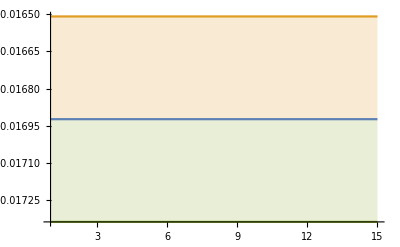

```mathematica
Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,15},Filling->{3->{1},2->{1}}]
```

```mathematica
SpoilHWFLOPlotN3=Show[Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,Length[meanErr2[[5]]]},Filling->{3->{1},2->{1}},PlotRange->{0,-.05}],ListPlot[{Table[{τSteps[[1,i]],meanErr2[[1,i]]},{i,1,Length[meanErr2[[1]]]}],Table[{τSteps[[2,i]],meanErr2[[2,i]]},{i,1,Length[meanErr2[[2]]]}],Table[{τSteps[[3,i]],meanErr2[[3,i]]},{i,1,Length[meanErr2[[3]]]}],Table[{τSteps[[4,i]],meanErr2[[4,i]]},{i,1,Length[meanErr2[[4]]]}],Table[{τSteps[[5,i]],meanErr2[[5,i]]},{i,1,Length[meanErr2[[5]]]}]},PlotRange->{-.03,-0.005},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]],markerlist[[4]],markerlist[[5]]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]},PlotStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau_{\\text{steps}}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3\\text{ (LO)}",Magnification->1.2]]
```

-Graphics-

#### QCD NLO - gauss

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={380,380,380,380,380};
NWalkers=200;
Nf4α1LoopBig={0.229421,0.229421,0.229421,0.229421,0.229421};
aList={1,2,3,4,5};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
csvData=Table[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"],{xx,1,Length[aList]}]
```

({mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.059410813995464, -0.06008450529673266, -0.06027319383272772, -0.0623487995300108, -0.06051135782728127, -0.06235882741792455, -0.06051697157531908, -0.06217328200749938, -0.0618162430434691, -0.058741842618350894, -0.05998665733700477, -0.06075050988657153, -0.057732002700823876, -0.057768590574315715, -0.05787036017653226, -0.05853319523260763, -0.05874038394786307, -0.0589050079165074, -0.06027010086338042, -0.06349338466673106, -0.058383799520184715, -0.05758271222132011, -0.05828894526756328, -0.056808534273173825, -0.055609113377075345, -0.05419454502155185, -0.05519213736734476, -0.05393270292915072, -0.054227167242965585, -0.05564147770263624, -0.05569754832407421, -0.057390281867942886, -0.05796482386080661, -0.057959997360301614, -0.05818315638105435, -0.056317493662500835, -0.05510319642959317, -0.05682076913732273, -0.05679616633604197, -0.05785433976557173, -0.0584735713831811, -0.06021837462635323, -0.06263497836071097, -0.05576679767635877, -0.05709115470594487, -0.05563551206605842, -0.05535037251321498, -0.057010676229745934, -0.0580318927745768, -0.0567108923086914, -0.05614934650161391, -0.05647911851014543, -0.055797474501080774, -0.056995061116338896, -0.056610138999697454, -0.05744092745473058, -0.05714344458922806, -0.05895568363250034, -0.06275206923710014, -0.06742535947631342, -0.060866954561359016, -0.059972283404253625, -0.06659169417780908, -0.05887146935559563, -0.058567518696843575, -0.05969951057944845, -0.062373619581067165, -0.059909265851589476, -0.06036576291688259, -0.058398304419968565, -0.059052805666959175, -0.06177951831936035, -0.06056496149909401, -0.06027419371018595, -0.06125621424782756, -0.061494902495167175, -0.06114288431047961, -0.06021148088263052, -0.06072088176979909, -0.060675699508160014, -0.061279815526937204, -0.06372011955267094, -0.061342291675169885, -0.061751153741846254, -0.06152209076418807, -0.061274220116582, -0.06206209117959135, -0.06188409485605495, -0.06430695010440453, -0.06141497133931354, -0.06344725481605422, -0.06460654085137259, -0.06840129085031142, -0.06837789242274708, -0.06838549456964607, -0.07068869830409648, -0.07285664882127053, -0.0755045292107704, -0.0691211327445946, -0.06883663983218946, -0.06470574555044539, -0.06771293251027413, -0.07020248478322416, -0.07388959430116894, -0.0692008097584739, -0.06699881595566956, -0.064880909548526, -0.06570488486116319, -0.06388560225954158, -0.06446617303154555, -0.06401045046605204, -0.062099074011559945, -0.060381779802592635, -0.05953235110125329, -0.05928665430032224, -0.06028039549228984, -0.05983386180652051, -0.06254031986709291, -0.06080019148872163, -0.06013598072467684, -0.05722251797804772, -0.058319109376449504, -0.05828211678468404, -0.05622929125984666, -0.05638977406548953, -0.05580401839174112, -0.054599941778068525, -0.05422733442537791, -0.055317940554992256, -0.057876121167368524, -0.05862229186788148, -0.05789291897919864, -0.059233496162014086, -0.06146654531889779, -0.06057888472779213, -0.06060586152428742, -0.059696350820628956, -0.06102044855109013, -0.06298547480557752, -0.06331293939914166, -0.06311159506940651, -0.06642478331768016, -0.06539060729617219, -0.0632196724212562, -0.068308019837823, -0.06619232368835881, -0.06706708458146121, -0.061058462838845765, -0.06090180697443708, -0.060940350786893874, -0.06095035016135329, -0.06072668275944145, -0.06265601947720206, -0.06655928245401063, -0.06104408720160655, -0.061921470364138226, -0.05974671439091164, -0.06278821416819258, -0.07509477566163025, -0.0694469604899953, -0.0700569374780137, -0.06343499544089344, -0.06246862368247721, -0.06242027738154777, -0.061415441102367734, -0.0629933854692324, -0.060461063049422066, -0.059799373511543685, -0.058933661030803296, -0.062432810792616714, -0.0616337744389064, -0.06060930058366343, -0.058877792739302055, -0.060371441074009415, -0.06235475265436167, -0.0612860510339328, -0.059278042086081076, -0.061913985159608845, -0.05922593682617193, -0.060684283876715095, -0.06097882207006152, -0.06143559817630689, -0.0598560252918747, -0.05886792043478638, -0.057920371172960096, -0.058809678954905686, -0.059035799457586705, -0.05848822463381645, -0.05769905921071706, -0.05851134230775049, -0.057740942198294315, -0.057285116816081054, -0.059110683927790106, -0.06084695868592274, -0.05992476744897386, -0.06286894225493714, -0.06341588338267883, -0.06436738953718585, -0.06791862288291163, -0.06814338394978839, -0.06535696031210741, -0.0656647456830651, -0.06660783078926227, -0.060899144459934974, -0.0637295265818782, -0.0637664374444124, -0.06238335680848156, -0.06261903885748098, -0.06057200016757456, -0.06157963639312971, -0.06635700547040721, -0.07019210662777023, -0.06630505508483264, -0.06073186398864496, -0.06482611884050939, -0.06551815443777655, -0.06917153108206771, -0.06513355631981245, -0.06315940319493059, -0.062348365632765565, -0.06165467442760902, -0.06494006641982569, -0.06453457164335301, -0.06802692306357246, -0.06796768285624769, -0.07830583799004168, -0.07432733900319057, -0.06519754076922515, -0.06537468741828315, -0.06667174765106217, -0.06686209848978515, -0.06310112518207453, -0.06828068631447354, -0.06572996278721613, -0.06518907568438893, -0.06770965069266303, -0.07118355623244942, -0.0687713132696755, -0.07091287692789053, -0.06692589530863692, -0.06606760984271902, -0.06526721590508372, -0.06899055178920023, -0.07911585325211339, -0.0738282043252764, -0.06583246133593694, -0.06313696282209402, -0.06542059582895494, -0.06714914787477273, -0.06556409368996713, -0.06461415830199366, -0.06428708146422382, -0.06527253867250492, -0.06365621628246582, -0.06590893489908485, -0.06799147304254441, -0.07665477948146533, -0.08638509808750638, -0.07637834953147649, -0.06906223338520927, -0.07292085883116943, -0.0741734734630061, -0.06938910962211206, -0.061232177280131715, -0.0650071743513334, -0.06878554486798011, -0.06846559721488037, -0.07089207825673272, -0.0678445697749022, -0.06626052104429633, -0.06380920914649832, -0.06210015323098616, -0.05925938075938093, -0.06093274645257224, -0.05822718007510203, -0.0553732988111919, -0.05846461577078376, -0.05497540321314584, -0.053388543261772295, -0.05477392919336178, -0.05251492261639221, -0.05189765215955477, -0.05296421616748256, -0.053025578570825814, -0.05394787414099306, -0.05368874370113353, -0.055307564357149334, -0.05819546820929909, -0.0553606839017441, -0.05589073935374304, -0.05651537871247264, -0.055843292622916214, -0.0545168193805939, -0.05547299664088496, -0.05437845440632416, -0.05388779718807166, -0.05327129495715862, -0.05476912192738434, -0.05487730699507293, -0.05494404405865526, -0.05472123125206329, -0.054557912956675246, -0.0578757102432879, -0.060086486512210095, -0.056708040648581336, -0.05875991786265833, -0.056871091421374864, -0.056108068169415416, -0.05566018189538518, -0.057432226499178084, -0.05782827368962661, -0.060989935940085956, -0.059277038661699, -0.056267312708984156, -0.056142699723535756, -0.06057490067060905, -0.06440764039278657, -0.06633762005092944, -0.06395058247674214, -0.0635850646443947, -0.06039963214701827, -0.06878313605471834, -0.08591880036699923, -0.09509479885839202, -0.08670009021852648, -0.07377365711061078, -0.09456104474590604, -0.0725305580529811, -0.06865416294695019, -0.06822432500278926, -0.0649677976483057, -0.07012005019163496, -0.07472921066546166, -0.0811375960436783, -0.09204885938433688, -0.126757038587884, -0.1050026521637843, -0.07487265018792069, -0.07134441970691893, -0.07034274982155629, -0.0729033755797822, -0.0755213806098428],[0.002305371233908121, 0.002402442801818292, 0.0023555611317906044, 0.0030175299431675754, 0.0029604119349570255, 0.0043924693650333555, 0.0032797881527251854, 0.004874905095092133, 0.005910429204620268, 0.0030886196921632854, 0.0036938525505200814, 0.004171530154640384, 0.002024322392362591, 0.0024503230109242696, 0.002471266892801499, 0.0026630951492357694, 0.002479663777336349, 0.0025452285258543883, 0.0029924244260769203, 0.00643835192992072, 0.0025631674665906362, 0.002249342958849234, 0.0026107955831589894, 0.0021589075879712015, 0.0020133522470588486, 0.0017434383632449243, 0.0019457514427176869, 0.0019187846825859983, 0.0018195244555079416, 0.0020898133310505744, 0.001812554284299259, 0.0025453703091206197, 0.0027647629764949765, 0.003008581344066583, 0.0027144414087209054, 0.002229962593665726, 0.002424705240773844, 0.003023152906587406, 0.003009832334841388, 0.0029247546102876207, 0.0037602931764611426, 0.0053213118166951226, 0.008129638204375405, 0.0028698021508126092, 0.0036969131381844695, 0.002573074590164589, 0.0028239782581900843, 0.002872441977044344, 0.0035133466930131604, 0.002744681413140791, 0.002699403283221473, 0.0032947410748453486, 0.002562454989983824, 0.0026058736217953924, 0.0023253486617443395, 0.002587419480245226, 0.0024207321011907317, 0.004072292464801373, 0.0057046103538982125, 0.009630673225149657, 0.005070717512514111, 0.005068393069727874, 0.011589567484656293, 0.0033297339811640576, 0.0031774720085077602, 0.003499744611474834, 0.005400838601465225, 0.0039298560421342135, 0.003485919536724965, 0.002832920471226482, 0.0028964395411384155, 0.0035843285399744336, 0.003315762141326613, 0.003126010603720578, 0.002850420652328373, 0.0032347806799620953, 0.003283058655945487, 0.0033165013913891853, 0.0037817553486624873, 0.003935149634473263, 0.0038895095875315527, 0.004400405526470968, 0.003620660273051919, 0.003934216076833429, 0.004059360070821379, 0.0044073331531965165, 0.004622199197899862, 0.004538907349498935, 0.004902521811426085, 0.004494378513433085, 0.004780590808489834, 0.004934053034727376, 0.005799489481872246, 0.005811633709151818, 0.006348024717269656, 0.007665852581604362, 0.00858708970119512, 0.01233072360930424, 0.005805447535815938, 0.00712743946813221, 0.0046069071433850915, 0.0058488413577106445, 0.006939694824074575, 0.010450018424921657, 0.005530963812724432, 0.004335623311634719, 0.003966159729196279, 0.004087294743000605, 0.004355690452656747, 0.003834575451059718, 0.004045511774058602, 0.0036141317579760617, 0.0030464385438372216, 0.0036178830943652224, 0.002960672847889895, 0.0033062915021329475, 0.003021624705975994, 0.0037102058000665415, 0.003701383488653474, 0.0031854596284989485, 0.002364067923766894, 0.0023840321641086896, 0.0024332297183648375, 0.001961218133183701, 0.0018819210006366088, 0.0017601237053411372, 0.0016882656786129822, 0.0017118574369688758, 0.0019161723340137213, 0.002731926815246178, 0.0029382712256484267, 0.002715114262243149, 0.003243538769729969, 0.0034344372737380377, 0.0025997535822484537, 0.0027224980483836667, 0.0029689766918500195, 0.003480920446276661, 0.0052720469573767454, 0.005913229587563804, 0.0049771581981702, 0.005509263739910884, 0.0049052725342360335, 0.00440603517231738, 0.007589782812825892, 0.006275381481442419, 0.008848883765282506, 0.004295206428290809, 0.003649563503160213, 0.003839398558787983, 0.0035542256750041505, 0.003250711760127305, 0.005167470362631258, 0.01008980753252341, 0.004720843778168715, 0.003974394642201831, 0.0028855282768804696, 0.004681174786788624, 0.017148197666517564, 0.011025292903048909, 0.010012637460165664, 0.004716319077819758, 0.0036731376048574934, 0.0038573251633674754, 0.0030204492990333507, 0.0035669005088890785, 0.0029600663789712254, 0.0029191593798992724, 0.0028352971369235195, 0.003995691813293283, 0.0032619891176743922, 0.0029149372726887746, 0.0023546871525796293, 0.003048737877912837, 0.004053124996129132, 0.003265299611946232, 0.0026563387323096203, 0.004999988871173488, 0.0027413682286839564, 0.003375370037581032, 0.0031489241848343718, 0.003101730931694069, 0.0028349757913232656, 0.002362021682114675, 0.002461165580306516, 0.00342808689500105, 0.002455411085288732, 0.0024054350757466655, 0.0021485897559221185, 0.0024983588926196466, 0.0019284146557990785, 0.0019621194207675883, 0.0028177620458431024, 0.0030527477965188016, 0.0024837437168270873, 0.0037915064674657003, 0.004160351753655797, 0.004192506047510049, 0.006358887756501925, 0.005560683670961482, 0.004785497038676143, 0.0044300375970436545, 0.004285921879104563, 0.003026324503416969, 0.004238223224847923, 0.00402880110867341, 0.00332968029247227, 0.0035086866206183644, 0.003499267906433973, 0.0034155387613745815, 0.006034605504737197, 0.009188574019058657, 0.005802915189409686, 0.0031760320070169067, 0.004704949454892013, 0.005450318910290222, 0.0072671853983888295, 0.004956903217888423, 0.0031580617923163017, 0.004124799867165795, 0.0033989021304153986, 0.0055440998875858965, 0.006738489004690566, 0.00951538116128207, 0.005956714650441917, 0.013501660874644938, 0.008418686986185225, 0.0047801404400190164, 0.004628152396883132, 0.005229105507382392, 0.005387760338341177, 0.004926400778908812, 0.008289765731859577, 0.0063545789688261925, 0.006282140009408906, 0.006677936302538353, 0.008797114340565185, 0.007137970431271005, 0.009085995574657783, 0.008159093447170486, 0.0071840133461323966, 0.006044475387005239, 0.007951459852906868, 0.014714178161394486, 0.012473090367385567, 0.007245056826255657, 0.004344211857615661, 0.0052794995563470015, 0.007007056574424828, 0.005990404412250526, 0.006177026830126086, 0.005475364831002891, 0.006390862526526971, 0.00494817116969893, 0.005963205217100811, 0.006845524747223982, 0.012043629909164246, 0.02305141638829888, 0.014255569759765701, 0.008808451856321406, 0.010096826053173578, 0.01267988783124966, 0.009857010802312554, 0.0044694928672689435, 0.005760548268794758, 0.008520566605515109, 0.006955134644450231, 0.008477516333436647, 0.006167822996798201, 0.006526045952619342, 0.004572182632052998, 0.00356310848363359, 0.00320586484216884, 0.0037919841760529456, 0.002557888878140703, 0.0022536402449613822, 0.0053629954080979415, 0.002838568487562264, 0.0021979904052058315, 0.003511224504831596, 0.0021306907960812636, 0.0016662834721177051, 0.0019999194509633745, 0.0015077814152878362, 0.001804469314811178, 0.0018578707451080152, 0.0026451419239931135, 0.0031096014782499844, 0.0024681586617567646, 0.0028400641073017215, 0.004287096147093395, 0.0032020842901972586, 0.0025555257368025212, 0.00258983211625815, 0.0018782722747099458, 0.0018593046425738101, 0.0018607937224263457, 0.00230197477602635, 0.0022203605932563254, 0.002566902435232761, 0.002144091745396145, 0.0018435011558208035, 0.0032871291857806775, 0.004042337851297767, 0.0023332397514901643, 0.0032057676363060556, 0.002353715204459952, 0.0027247513831648437, 0.0027550783422800444, 0.002947656367370153, 0.002947387253505257, 0.003906713420968079, 0.0034655927159278166, 0.0027378791534591464, 0.0021219862805998617, 0.003997837870970262, 0.005563124328893887, 0.0053929382240508646, 0.004731408489842301, 0.0048475598807863575, 0.0037687728440671427, 0.008406686155783926, 0.024442014379082774, 0.03317684853308574, 0.02478150190552879, 0.011032461894448908, 0.030220487564580144, 0.0108218325727981, 0.007233790407210621, 0.006955856736927309, 0.005225595715519718, 0.008239140744722992, 0.011732975770934968, 0.016299076579220462, 0.019509935989998974, 0.05085756230813492, 0.035423012013532124, 0.011353307159541299, 0.008579133451668284, 0.00811036480699099, 0.009529549979008055, 0.009976106247965372],-0.0560764,0.00034982,0.531796}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.04961926785753087, -0.04875838199051992, -0.048865167068621505, -0.05013989733705081, -0.04984646752420883, -0.049538270001240885, -0.04969094460724824, -0.05048486558272966, -0.05026116574330431, -0.05091577307347683, -0.05149166132621642, -0.052613660751697995, -0.053094662415046824, -0.05160953007155179, -0.05209577145457499, -0.05124112891755292, -0.051352713425968595, -0.05166683896632895, -0.05260805181109907, -0.05369577333190729, -0.05374800410784172, -0.05431800640474943, -0.050820018991208415, -0.05114708457785244, -0.05064435892287312, -0.049940304342693954, -0.050190959006427435, -0.04876215654196407, -0.04863787067703664, -0.04851145221649733, -0.0495230442433685, -0.04956824606971551, -0.04966106983786995, -0.050577692121545656, -0.0490521614425917, -0.04859571722858274, -0.04924625068872602, -0.04931311897344464, -0.0499458112094802, -0.04986887907707052, -0.04946334054513867, -0.04993528631849531, -0.049258677899157464, -0.05083284343952556, -0.05085171292067949, -0.05155726180559732, -0.053243576988604296, -0.05366741555523069, -0.057126013233835156, -0.052431210050081806, -0.05025656576996771, -0.049994712833100315, -0.0493779530766608, -0.050570816019694674, -0.051058624217561924, -0.05089211064545283, -0.049198476298065404, -0.04866332099893578, -0.04929446965216544, -0.04778053562326279, -0.04744938064940355, -0.047294234769505596, -0.04820970813548383, -0.04806975687349486, -0.04803249260416406, -0.047768376799681045, -0.04777330002095556, -0.04872507880856027, -0.0483334525775743, -0.048451619305769744, -0.049135353575224756, -0.049166354128704966, -0.048671535800093195, -0.04850038263060225, -0.04874179126518214, -0.048864154135440964, -0.04875266877862654, -0.048380692890915664, -0.04805984801246078, -0.04710224135248059, -0.04817968409926527, -0.04943232422584237, -0.04873287070287648, -0.04884709643964295, -0.049323747398663485, -0.04910219711585839, -0.049557843675413264, -0.05018280238083145, -0.05139013023594673, -0.051217444633662616, -0.05170135471324581, -0.050365998766775104, -0.05082590354926137, -0.05031336891364089, -0.04982051840721701, -0.05053373934509492, -0.05165767963612005, -0.05242031416991714, -0.055438417267509595, -0.056867878541419045, -0.056398867982916046, -0.05885150076922539, -0.06234363214489568, -0.06198556787254981, -0.06401364273393552, -0.059247559847852835, -0.06252336325526461, -0.05856147911411508, -0.05666507905140783, -0.056195251401130644, -0.0566103991253953, -0.056048627613939694, -0.057152225794050375, -0.05784684322165864, -0.056156129707954285, -0.054899059034571665, -0.05290823362742977, -0.05267368332188092, -0.05278347344907412, -0.05242020394426675, -0.05116699222526408, -0.05206252974186771, -0.052375903732427335, -0.0524528351980067, -0.05396781252346525, -0.05330229097648025, -0.05350020049526644, -0.053140440292091265, -0.0543301963006418, -0.05554486096796573, -0.05752268448897101, -0.05433242291007152, -0.055216817510639005, -0.05667345141368702, -0.05666752489880592, -0.054729182229725316, -0.05443045839208484, -0.05309707224620838, -0.052912989951915186, -0.054285384780266406, -0.053454333311957675, -0.055215066781811005, -0.05364719874118119, -0.05434119777151389, -0.05301378715439149, -0.05151788994653251, -0.05021697500733884, -0.05204575576948068, -0.05292458623893968, -0.053441576605927056, -0.05284443795219241, -0.05333601535286509, -0.054286025343586654, -0.05299270061525659, -0.052215283713801436, -0.05300648516287256, -0.05373935526927685, -0.05483275281893926, -0.05430326218914383, -0.05342858864130025, -0.05312119959403525, -0.053545373024138, -0.054848932182535066, -0.05544287365271275, -0.056637950758916256, -0.05539144903644662, -0.05495598544442953, -0.05797400689051886, -0.05681837971264729, -0.056648376580452686, -0.05596496441050808, -0.05688355381640251, -0.05432452495378278, -0.05425728003040745, -0.0549224877555762, -0.054566492793997445, -0.055462345346563975, -0.05678827877554646, -0.05834614267221954, -0.05677344579587926, -0.05649067691581981, -0.05502682913686812, -0.05538882297427583, -0.054715371210538266, -0.0553949108374451, -0.054272778504892004, -0.053102006222202784, -0.053200452049856316, -0.053304586649738195, -0.05406267249009467, -0.051972240044664386, -0.05169992925753643, -0.05155683386652852, -0.05096232707773074, -0.05051161209840607, -0.049584227539599464, -0.04948348444513885, -0.049921475923120864, -0.049930768119823096, -0.04972960003681562, -0.049861088765179855, -0.04937605553759836, -0.04870948233669845, -0.04905380649288423, -0.04858335524320622, -0.048388856455667775, -0.04943783627745964, -0.04913087074570902, -0.04824607087251684, -0.04802374132306783, -0.04770136186472727, -0.04852644324209525, -0.049516070166511494, -0.04907051002402215, -0.04800515205930925, -0.04776498553531698, -0.04746756396674746, -0.04764901590253755, -0.047885416924166944, -0.047833832163528475, -0.04855355466491568, -0.0505744489382346, -0.049577551648553986, -0.0486584116037696, -0.05005213059153291, -0.05163725622414116, -0.05040953164447331, -0.04927887907775664, -0.049595643446959554, -0.049896056353107975, -0.04886297178777028, -0.04762776889948168, -0.048205643279020424, -0.04774889670798639, -0.04871998556484781, -0.048749408733587414, -0.048430408994301476, -0.049514924740457, -0.05018671952353206, -0.051372084618371804, -0.049370314862844836, -0.05078701565336426, -0.0517015529203229, -0.056181160665476945, -0.05273164418717917, -0.05541200154306622, -0.0521582605563962, -0.05756464250698712, -0.06001888890742922, -0.05654790599026839, -0.05264349258095085, -0.05281748966281946, -0.053340347638537906, -0.055062215512495474, -0.057380361634772295, -0.05880229652022076, -0.057352474598969784, -0.055768196905352736, -0.055472862028494954, -0.05476489912694798, -0.05499747214637956, -0.05703864083794429, -0.05500214541442237, -0.05331716393174816, -0.053001539606751316, -0.05440456773369121, -0.05268246944012347, -0.054802397748185704, -0.05411190800579313, -0.052619100288191445, -0.05270247716137619, -0.0538643145177963, -0.051174671251204236, -0.05102778015543329, -0.05190639638114986, -0.04894328257363113, -0.04931928429243448, -0.04841907083997504, -0.04996390516002278, -0.049224400622918975, -0.04992780608007294, -0.04903923164747816, -0.04809898057965684, -0.047561791790795, -0.047915985409554454, -0.0485741263019072, -0.049936007905728004, -0.05207869197740267, -0.05054517491276164, -0.05004039424539376, -0.05030772545409686, -0.04909353209162222, -0.049120870622790504, -0.05018373779909701, -0.051541716071925946, -0.053352211437090014, -0.054180299691443855, -0.05410347138652333, -0.05454326466236047, -0.05491076989111278, -0.05371198883714727, -0.05393929353613615, -0.05301077479708468, -0.05374565079290336, -0.05386123936652777, -0.05434139530415215, -0.054399927173880994, -0.0563396558401032, -0.05551193491503249, -0.05241457245032294, -0.05352971826535172, -0.05346815718069903, -0.05213732553243397, -0.05126153323372356, -0.05015067127894087, -0.04993500527081459, -0.05199627416073749, -0.05305660466017402, -0.05079936595779153, -0.05011877146135103, -0.05265591346292631, -0.054442385145033176, -0.05534387263863543, -0.06001214242459601, -0.05988007968413196, -0.056558966117332445, -0.05653953812502878, -0.05522187775550648, -0.05432497903621623, -0.05199808550209288, -0.052010896527764916, -0.0532442249128072, -0.053766815175747294, -0.054252231034829616, -0.05634642693934885, -0.0572171940043547, -0.060010875981246464, -0.05357557892119328, -0.0541778163028911, -0.053229391658009856, -0.053141375157333436, -0.050418119737326156],[0.002991584847716345, 0.002405103204588087, 0.0024533971896277046, 0.0027427659874763757, 0.002701838854047639, 0.002479781748207869, 0.0024409742789213104, 0.0027179570822882834, 0.0026939670773691846, 0.0029156116835866615, 0.002661593330733677, 0.003100274377994397, 0.0038990507261686524, 0.0031091964445995116, 0.003465261659807875, 0.0028205878276231218, 0.002840848492667961, 0.0030196941536256143, 0.0035010575316684876, 0.003987584792212024, 0.004117653691762955, 0.004372016051474112, 0.003112715959828008, 0.003221962879458503, 0.003034656987054652, 0.002868380333210807, 0.002822505378000732, 0.002416479241095801, 0.00254450768836232, 0.0024558197622115384, 0.002645070476386991, 0.002749196399380896, 0.002814810366549903, 0.0033810094651320014, 0.002672877980515155, 0.002439030162591248, 0.0027418370591532817, 0.002679979141367172, 0.0031142825248046554, 0.002818630033408961, 0.002520660374043505, 0.0027708089293638333, 0.0027558535975365957, 0.003335596647277813, 0.0031296272555810236, 0.0036441673186700958, 0.004766910063850041, 0.004726445685775467, 0.008055155612410162, 0.004558784075223928, 0.0033562169321678863, 0.003084333085225022, 0.0030869178599820784, 0.0034188970150040585, 0.0035501101270492426, 0.003172128976074107, 0.002275310049520278, 0.002273688875984918, 0.002337302731344913, 0.0020744499571619993, 0.0018484467672074691, 0.0017559820300482238, 0.0019762594475793414, 0.0018058751945627194, 0.0018253259005117613, 0.0018549317404838385, 0.002020580691000699, 0.002256567850499621, 0.0019890804293930774, 0.002006298509825177, 0.002367278226187024, 0.0024193970017372213, 0.0021713076237629293, 0.002031200385608707, 0.0019921898501861113, 0.0020347738520128827, 0.0022222226360493324, 0.0021883714903308264, 0.002170773834968876, 0.0019344214298821698, 0.002282746151371608, 0.0024847743723936323, 0.00229956318788986, 0.00229367058022001, 0.002607160839649264, 0.0024224155378820425, 0.002613775989692113, 0.0030880583485270274, 0.003459069005306913, 0.003410293277856436, 0.00383241975823215, 0.00312240735436233, 0.003324814439132911, 0.00296066889686846, 0.0028277016050490635, 0.0031767941285978617, 0.0036018060991118432, 0.0038665511300084625, 0.004991237438004343, 0.005839476011947889, 0.0056710218518585395, 0.006634091836868055, 0.00939730749244741, 0.009068119001239855, 0.009767491556418649, 0.006874829647967886, 0.009582396336573236, 0.0059871265363205285, 0.0049274303758703964, 0.0043236147308860365, 0.005146632715621276, 0.004815262594148588, 0.0052522108895048875, 0.005285318265064897, 0.004780139602984247, 0.004022893930861396, 0.0031122297038887695, 0.0028824249726296172, 0.0029573929909833515, 0.002675474603479282, 0.0023468791938549235, 0.002420268789344128, 0.0025486038874589904, 0.002604271882485077, 0.003167464919541164, 0.003021627265106266, 0.003038114932646481, 0.0030342387724375665, 0.003697576591877383, 0.00434398756106222, 0.004962050629662973, 0.003367170125153746, 0.0034061005101493247, 0.003812738141747232, 0.0041769510411497675, 0.0034255114985178997, 0.003466042941498993, 0.003441928473751563, 0.0033257334866971613, 0.0037043243593168464, 0.0036157330287454365, 0.004337134228818587, 0.0032457493970449863, 0.0032571810379414734, 0.002747308395590014, 0.002220966630287489, 0.001956675565900631, 0.0023030236800480716, 0.0027438867454580274, 0.0026261984313997884, 0.0025495507687115426, 0.0026049557225389305, 0.003198633743746548, 0.0030034003914316846, 0.0024434105351216597, 0.0028334365651994705, 0.0029262242008573887, 0.0032964363109359227, 0.003135999066418626, 0.0028669088327750256, 0.002759349118300677, 0.0028016468170488436, 0.002840417720043256, 0.0029095928171961757, 0.0032992802643882556, 0.0031661761167136836, 0.0030488621649653624, 0.005015873711455987, 0.0037543605189450054, 0.0042011937477361054, 0.003493799014372236, 0.004375462385954644, 0.0031428822566059544, 0.003069652258408627, 0.003202213493215604, 0.003198862677328525, 0.00330928213876104, 0.0038184407062103014, 0.004255734372320853, 0.003779483551114857, 0.0036736062512566885, 0.003231702781347893, 0.0035678498321724083, 0.0031730721106471567, 0.00324774797594671, 0.0032841858255457114, 0.002825088090552672, 0.002858852195352328, 0.0033403277415974516, 0.004036597100473115, 0.0033404973490956122, 0.0030153041997268318, 0.0027494583085126067, 0.002447698364374391, 0.002705424330685325, 0.0023825816087765022, 0.0021233905595869204, 0.002439398637307293, 0.002327934836831805, 0.0023797096581208398, 0.00223694024873555, 0.002097464228609306, 0.0018724732220577437, 0.002018999140889206, 0.0019866516519785613, 0.002138405045817548, 0.0026334709096992115, 0.002313503152982387, 0.0020895503787291604, 0.002455354632254103, 0.002284834774785357, 0.002823835230046941, 0.003496021137591646, 0.0033657286627764844, 0.0026465215280584878, 0.002655344652083126, 0.002527675600246975, 0.002676771140459181, 0.0028562722220560953, 0.0031483569135364693, 0.0033238443755463937, 0.004069873015153459, 0.0037344058850649767, 0.0035388775307418083, 0.0041866618059000285, 0.00496774109002602, 0.0040488728472635625, 0.003451053537756556, 0.003654590983153663, 0.003736516916360456, 0.0034485471712136164, 0.0029649658132981176, 0.0032900824356046896, 0.003000245790433922, 0.0033320637597092613, 0.003546561513106105, 0.003344046553090029, 0.0032100093742538963, 0.003382050364578869, 0.004360256367249993, 0.003281795277757181, 0.004308207221456216, 0.0054597430891672885, 0.009428522044058666, 0.006125908495409338, 0.00862943446259116, 0.0056308635606872786, 0.0104750505988304, 0.011839082861977332, 0.00873468205645678, 0.005776875870688864, 0.005202159688854406, 0.00484095757527482, 0.005430559124454912, 0.006352586836052387, 0.007200005139084146, 0.005887191394026238, 0.004932451682006285, 0.005101617634798472, 0.004854850769869636, 0.004679080062504257, 0.0065094105709946025, 0.005248688254369249, 0.004671340255999358, 0.0041216574240692415, 0.00486407709859984, 0.004005460790947816, 0.004925377391715076, 0.004329021429340254, 0.00398301064103145, 0.00393758519653736, 0.0046852200720145344, 0.003240387622636734, 0.003245895151534401, 0.0037207215251013827, 0.002645030130491214, 0.002853286656731263, 0.0024278197598641754, 0.0026209498778430886, 0.0024646101036454437, 0.0027864279938030058, 0.002738872436799036, 0.0025767794654614814, 0.002523070017683239, 0.0026686855976553116, 0.003064813309695338, 0.0039933026711689796, 0.004883418622893858, 0.004446631285414188, 0.0037673475982337046, 0.0038723918169744163, 0.003375139277956367, 0.0034311156739292026, 0.003938933983464108, 0.004384404324412475, 0.0052115589775323275, 0.005478592967330754, 0.005778285888551923, 0.006093409936719845, 0.005689874034635265, 0.004928338015857714, 0.005018651637622502, 0.004841343985748099, 0.005086204742372479, 0.005216675523532812, 0.00495474721553242, 0.004779748973153174, 0.0062217397521251196, 0.005659059456682462, 0.004031316949220585, 0.004698332365773392, 0.004483675426480019, 0.003999166831785062, 0.003685841026689426, 0.0031091888440490287, 0.0029451413077496796, 0.004156766398276214, 0.004644768761753579, 0.003625479974399187, 0.003970231833669082, 0.006294481927161927, 0.007827960844958777, 0.008014576115765407, 0.01079810695569275, 0.010971295230480491, 0.007804831020486907, 0.00742375818841671, 0.006279835612297567, 0.006016665644609122, 0.004733869579854486, 0.004832055918594632, 0.0056007544164321695, 0.00582692051939452, 0.005920779382058182, 0.007627484291465789, 0.008533031619395656, 0.010770214482227062, 0.005216743299048548, 0.005775754398917697, 0.00499638178203354, 0.005016051314269121, 0.004056102027219058],-0.0445154,0.000661415,0.312251}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.032755861597859245, -0.0329991268511762, -0.033241573175038897, -0.033268840012498364, -0.033940843700074566, -0.033704846184928805, -0.03514488652986961, -0.03533425399017599, -0.03513706718156513, -0.035499470390316756, -0.034946824209968405, -0.03443559423275805, -0.03438565205682844, -0.0339555783207181, -0.033777217854587704, -0.03338189358307345, -0.03308782223158193, -0.03320131695602286, -0.03336350354613903, -0.03338662080380092, -0.033508311799193995, -0.03338932791000797, -0.03359676084490894, -0.03366718019666893, -0.03339783626304673, -0.033213849678785455, -0.03328544626205096, -0.03321464832160989, -0.03307666775255622, -0.033201703030221755, -0.033260888217353284, -0.03336449868533483, -0.033799668563053595, -0.033994600602223354, -0.03430171788199857, -0.03440441405414038, -0.03445647421862629, -0.034718253433988766, -0.034679286609386836, -0.034698161626344266, -0.03483682417455465, -0.03418647779974833, -0.03431939361314079, -0.034638207650580684, -0.034445447030002706, -0.035017277553766324, -0.03458421153012805, -0.03427117886291141, -0.034865271927037755, -0.03491541112013832, -0.03542945021189329, -0.03530999211200759, -0.035407186866088666, -0.03564668006088443, -0.035417075916179305, -0.03589609010663591, -0.03563546551264741, -0.035563220356263296, -0.03593165052022929, -0.035994289095392026, -0.035563387614104325, -0.03531761794170554, -0.035406876533996864, -0.03570431685661205, -0.03584594873006065, -0.03580601015584989, -0.03563059371178239, -0.035878919580893495, -0.0364805560407298, -0.036620958789804606, -0.03657705077667118, -0.036700394005276735, -0.03699962858793918, -0.037730533461750274, -0.03865499414044684, -0.03831977769079991, -0.03787902622514354, -0.03820551578801348, -0.03784489737639441, -0.037577555215868454, -0.037996309325396466, -0.037950878275602215, -0.03773601790237123, -0.03766149117666554, -0.037821989939299416, -0.03766162277913003, -0.03775637611419333, -0.03775707100995623, -0.03710271615787697, -0.03728738958729441, -0.037753597347986716, -0.03798654188838207, -0.03765111610535803, -0.038250982301575094, -0.03769907831460446, -0.03804974061589014, -0.03851256002747411, -0.03853886601168943, -0.038673172029195034, -0.03817481520547123, -0.038645261788333087, -0.0392424298800591, -0.039273905599967254, -0.040263459112398016, -0.040418976160965424, -0.0396939976365104, -0.03965043233982667, -0.0389063844789758, -0.038219294718871324, -0.03804410856392683, -0.03801932118250318, -0.03816747808171542, -0.0389978954892978, -0.03918395943859547, -0.039879459874853716, -0.04032138034928497, -0.03985247943494019, -0.039368549351314966, -0.03934753450548862, -0.03979219259461211, -0.03947622790787282, -0.04022093187185892, -0.04060785262388107, -0.040746312650975614, -0.04098898281558222, -0.04088791870559678, -0.04044652487569342, -0.04075636982598695, -0.04117695703384642, -0.04130536985444435, -0.041672215718797645, -0.04241790307100753, -0.04344413834542411, -0.04392667859142987, -0.043986445583707755, -0.04386123429794208, -0.044230034269541904, -0.04380448565662277, -0.044712477342054725, -0.04513133293635752, -0.04481118580820724, -0.045394900912764394, -0.04629955521042284, -0.04664857706588793, -0.04540291275392944, -0.046229091921858805, -0.044747569112665565, -0.04491776208543829, -0.04406318661598636, -0.044542001672181177, -0.04371955753215344, -0.04578958358599061, -0.046151096485319495, -0.0466180688236287, -0.04480779353625268, -0.04534154550862388, -0.04572872127085738, -0.04612385058711869, -0.048144034615371555, -0.04580560992432611, -0.04393921861014295, -0.04392701229236771, -0.04480487576827637, -0.04491291335347129, -0.04656619850944138, -0.04593424642491202, -0.04626080082952249, -0.044615574161919296, -0.04514636144107992, -0.04489719439099503, -0.04585455446083256, -0.04547360278673411, -0.044523597028738406, -0.04327371555798926, -0.043729063536912305, -0.04250551741391634, -0.042807197949281374, -0.04344920385117111, -0.04324887130632196, -0.043567215751096455, -0.042821521042447325, -0.04279347734519213, -0.04295459096088541, -0.04247900150356651, -0.04230830301874111, -0.043154908622485944, -0.04368610695233158, -0.04345651224021927, -0.04261836710195803, -0.043383501159563985, -0.04328547643284533, -0.04321523584068607, -0.043423006643957957, -0.04343770090590932, -0.04278012508447573, -0.04368860187915832, -0.04413692469585156, -0.043693736891094896, -0.04394696560217812, -0.042970178734509486, -0.044485654839496215, -0.04417224660466724, -0.04412667321873892, -0.04567051059126721, -0.043887155853953995, -0.04341692955438914, -0.04439938980960455, -0.04566213810453528, -0.0454612190893513, -0.04581842167947697, -0.0455281933579255, -0.04593119800574607, -0.04523765636560404, -0.045480465005832416, -0.04745758055493227, -0.04639545622030737, -0.04700453555740427, -0.04935232818445738, -0.04810302094591529, -0.04782698766529416, -0.046701672898002373, -0.049633128630002146, -0.05159701976720421, -0.05158651391915421, -0.05288491982514891, -0.05150128787410356, -0.05180285273795154, -0.05154886840339759, -0.04924998328140561, -0.048639076535974005, -0.048378680852767315, -0.049836066462787494, -0.04956955931483537, -0.05390914614024725, -0.05038738930130924, -0.051511042026769614, -0.04983171475207869, -0.0486463804180028, -0.047158770417141976, -0.04821743681861247, -0.04834674329105041, -0.04930014841134136, -0.04913633218197112, -0.05005453771146387, -0.050753467149308486, -0.05342879158627935, -0.05444774769099476, -0.056742770151209154, -0.05457785176233725, -0.05303844087923214, -0.05203939549289216, -0.05329343452143641, -0.052931921080409346, -0.0540266675297834, -0.054104116393766555, -0.053655159137445445, -0.05357356347081996, -0.053920180631330174, -0.05682748594383928, -0.05322929894374984, -0.05692738458561868, -0.05705060396657725, -0.05701716697098344, -0.05595931933670236, -0.05741466017178382, -0.06430656396223437, -0.058471842163504754, -0.06326930973972768, -0.062436245833909214, -0.060836950660808166, -0.058022416097122144, -0.054207036252442865, -0.05391210090689209, -0.05359033482401303, -0.05523722785731252, -0.05101397794105375, -0.048562658355725014, -0.0491873296452425, -0.04938786413125253, -0.04967468508446979, -0.052562084650127225, -0.05253165630466518, -0.04874473002606137, -0.048517005244656304, -0.047819383530204276, -0.04681185767677471, -0.046999024942948796, -0.04545571083604299, -0.046242947435314166, -0.04581377516344594, -0.044403978732533086, -0.04347543105219199, -0.04449310492300552, -0.044253267259562405, -0.044494273881266665, -0.04583166429706974, -0.04571649571561878, -0.04618651912960309, -0.04638322266511093, -0.04757074377901771, -0.04717740158077117, -0.046966980525086625, -0.04816234921902607, -0.047776245998345554, -0.04754059321357799, -0.04761330906367856, -0.04784487161006665, -0.048129884591499736, -0.04688507108127172, -0.047592325457429085, -0.049387021546649396, -0.05094839050054966, -0.04805103883005537, -0.04857594720380812, -0.04970203097182015, -0.04903724814508266, -0.049393325109572485, -0.05053900136979123, -0.05358228257874007, -0.05206157300318075, -0.049980664390631944, -0.05180235460647652, -0.05229385472068884, -0.05227687229731891, -0.052452502015077056, -0.05229048560825297, -0.052254615658847946, -0.05410750097919748, -0.054702437009096515, -0.053396229248000415, -0.05535266965303601, -0.05252604834757044, -0.052441773257839906, -0.05318710420067073, -0.05444956288115888, -0.0560673162534182, -0.05609926518736053, -0.057602277020677585, -0.05717179029641866, -0.05871598322632561, -0.062212300038051775, -0.06346280665142325],[0.0011900002906289116, 0.0012962223674933544, 0.0014337600675405964, 0.001461237193065443, 0.0017451679299730926, 0.001663980148834063, 0.002834372027408083, 0.0029168947398543785, 0.0025955174289910444, 0.002731250019571666, 0.002091239562315736, 0.0017704401886499265, 0.0016864202961598131, 0.0014787920041594157, 0.0014762148580276966, 0.0013357350411161257, 0.0012294833643319131, 0.001243231937408598, 0.0012504107237904475, 0.0012829735591445093, 0.00130296823297047, 0.0012591151052716092, 0.0013695661084088201, 0.001368966189466169, 0.0013126157059754743, 0.001238160974008474, 0.0012746338457121798, 0.001226497700978948, 0.0011876630880515069, 0.0011637847091169572, 0.0011532100749977049, 0.0012069102438964012, 0.0013480098093957564, 0.0013937588034636803, 0.0014239815849890762, 0.0014473662183256224, 0.0014685150099406116, 0.001566698763497242, 0.001570925571600411, 0.0015246770849058613, 0.00157031108229434, 0.001378303385378362, 0.0015150875519020634, 0.0015430883579401864, 0.0014519475329511204, 0.0017128694229619607, 0.001583592256993028, 0.0014084978882255889, 0.0016022360517376928, 0.0015729265478141956, 0.0016714230911727258, 0.0017115656762322756, 0.0017087408069832407, 0.0017299146906698225, 0.0016313771469880292, 0.001754758134934486, 0.001639161203220843, 0.0016679449553491114, 0.0017508195969058215, 0.0018196191294042225, 0.0016601278866748743, 0.0015781008564856227, 0.00161552996390227, 0.0016375410977054578, 0.001701363531529246, 0.0016988841354344815, 0.0016212234916525565, 0.0017098150169966419, 0.001903395519412378, 0.0019466434005123376, 0.0018705827081137419, 0.001935098750586378, 0.00194437734485667, 0.0023877947360383235, 0.0028242583031406025, 0.002301914861851649, 0.0022196116747230745, 0.002459196620007313, 0.0023111331886299965, 0.00223878029304972, 0.0023472956101101596, 0.002238451280599809, 0.0021155166156784895, 0.0022408207793698167, 0.0023626068966248292, 0.002179450567068193, 0.002105129919506819, 0.0021620892214203585, 0.0019329367620997118, 0.0019770917511596534, 0.0021246093237086133, 0.0024298939578818626, 0.0022904224524599756, 0.0027027480630539306, 0.0023809114963445426, 0.0025544334405556307, 0.002641420955862607, 0.0027184417301879087, 0.0025098574811101447, 0.002205148208209496, 0.0025613082188157034, 0.0028111037962682533, 0.002754729876858339, 0.0033026238502778843, 0.0032942499614484473, 0.0026010766957732185, 0.0024911375740208695, 0.0021259421669978743, 0.001965456202222172, 0.001816124731446376, 0.0017966599177004787, 0.0018805008177189828, 0.002039312353949304, 0.0019736462354579356, 0.0022034342281446392, 0.0023670624419115894, 0.00231094050020389, 0.002253339017110343, 0.0022477136549360214, 0.0022852947665127884, 0.0021976694663111886, 0.0023482618988490424, 0.002464051491593702, 0.0025445936006387314, 0.002655876704784187, 0.0025372395046778665, 0.0024845414060446942, 0.0025765059714802224, 0.0026687050708056777, 0.002773280210320592, 0.002924235713180672, 0.0031604532884329864, 0.0036030615299617835, 0.003729583033425973, 0.0036960473302302733, 0.0037489140996024213, 0.0036259287729850332, 0.0036270799313704383, 0.004106745032463048, 0.004283549280943707, 0.0043714955223812905, 0.0046670324524137165, 0.005460079235107298, 0.005412605739075493, 0.0044629195859427675, 0.004843113311351667, 0.004038050248256815, 0.0042920946953106925, 0.004054911862101184, 0.004263199150436712, 0.003867920637851186, 0.0051016992099519, 0.005016446173770887, 0.00555560677635293, 0.0042212168088907025, 0.004206345628035179, 0.004535567674589675, 0.004768134902410994, 0.0072140973918619015, 0.005094600536393069, 0.003594874277413185, 0.0035450161843441283, 0.004275160749947612, 0.004403222276262133, 0.005674898052100348, 0.005840175261964966, 0.005983695472880356, 0.004173601938070954, 0.003955900418079958, 0.003964858268734536, 0.005036888370283828, 0.00458524976602356, 0.0036475875448372295, 0.0034458049274880024, 0.0036965556586401782, 0.003017699704381129, 0.00281586268271767, 0.0029901589130459775, 0.0027443689187670738, 0.0032596625503738064, 0.0028894158066378245, 0.0029571911685210045, 0.002962505615148183, 0.0023027665261278, 0.002240690067621573, 0.0025408905233480807, 0.0028711955688547675, 0.002749608508849339, 0.002539745417766034, 0.0026542574050013416, 0.0027016424957736415, 0.002707354846616748, 0.0027034409654471243, 0.0027947544191336726, 0.002521316651551421, 0.0029256480252023067, 0.0030204065267456395, 0.002644370586049139, 0.002857691154036357, 0.002673625073128619, 0.0035159058764770972, 0.0033663391403105478, 0.003146965429075843, 0.004001312960531934, 0.0032577511437271553, 0.002948695340635486, 0.00334336793923014, 0.004107445290955577, 0.003966136448239139, 0.004180030702347961, 0.004199278042374287, 0.00462091732146425, 0.004695046798588487, 0.005010461273916212, 0.006672811258666084, 0.0050635009111189, 0.005785494866312708, 0.007343601383795836, 0.0064221131957652965, 0.006182909203873358, 0.0050674991489986455, 0.0065250074528761, 0.007896937402664533, 0.008109713282712936, 0.008479569836880333, 0.0076134073544554355, 0.00786918456131124, 0.008172592618123796, 0.005905180062799218, 0.0056484388509163395, 0.006145281168339766, 0.007505742465656125, 0.0070847973146109, 0.010652450721669666, 0.007647246312161853, 0.008700224166870123, 0.006790115623796645, 0.005954704261424924, 0.004776680867341243, 0.0055778982522392195, 0.005916971226316459, 0.0071147376264479424, 0.00699118259877277, 0.007800361173162643, 0.00865499351044104, 0.011044832379529131, 0.011914540855796553, 0.01364206984330012, 0.011218363387829798, 0.010280603224978015, 0.008976526569316572, 0.009638985922925865, 0.009112339250894996, 0.009340817045033109, 0.008858246148308026, 0.008528040234727098, 0.008278360674812075, 0.008417187939680854, 0.009164239398736835, 0.007417261618277633, 0.01000839097358, 0.00951448486178955, 0.009978115242703908, 0.009470669441169, 0.009548445210634162, 0.01675681600650963, 0.012731395726672961, 0.016400975680994856, 0.01639392856934511, 0.014685495674688402, 0.01217390499476787, 0.00918601699863564, 0.0092916655988344, 0.009031376899745105, 0.010701315674628167, 0.007608915186271704, 0.005674890886228401, 0.005886792762447139, 0.005977035769840842, 0.006129164717546807, 0.008164764338080374, 0.008590437825735818, 0.0059186754151501365, 0.0059777571615607155, 0.0047884326127845475, 0.004489662517843566, 0.004209190486885647, 0.003614629190081463, 0.0041185639911289615, 0.004058205470312227, 0.0031704484273508055, 0.0028514254860065665, 0.0034219211821302606, 0.0032229064475397394, 0.003130610341525783, 0.0034227388357038167, 0.0032936001123584657, 0.003194953696803095, 0.0033866866272950335, 0.003695031632687468, 0.003636070362415001, 0.003498673439956223, 0.00390147665876997, 0.0034054204104439706, 0.003325589795420886, 0.0031205305308700136, 0.0032525238742955654, 0.003610602389418364, 0.003280320287802309, 0.003655032903701813, 0.004152879785712798, 0.004824214016540305, 0.0036223201910682875, 0.0038634124587174027, 0.004821487369442966, 0.004596836479105517, 0.0048279095145577905, 0.005534443579935011, 0.007839384301325202, 0.007186778759292232, 0.005417639640128455, 0.005716926462679555, 0.005784357456974543, 0.005360479391223027, 0.005192768335524665, 0.004769815461285299, 0.005011302133545733, 0.005827436116373384, 0.006030038498099064, 0.005389515611515856, 0.005827318201604888, 0.004745939813490635, 0.004777493885244647, 0.0051475703073978005, 0.005533726159196903, 0.006300970772159483, 0.006202109708158676, 0.00727600768314694, 0.007020226630878097, 0.008329103379236844, 0.01042830743453394, 0.012929422690945016],-0.0333371,0.000665004,0.261302}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.02639501399500796, -0.026743300509538475, -0.026886509272105064, -0.026663415939702652, -0.026741555108142138, -0.026688562362902638, -0.02655570671132608, -0.02653009212917049, -0.026647226330781978, -0.026828425497363646, -0.026944652190949624, -0.02656965101999414, -0.02671337728050344, -0.026635834891650115, -0.026509127324810852, -0.026519839400266074, -0.02654439496181654, -0.026540934793682372, -0.026905573363963965, -0.026878427494342688, -0.026806342155849323, -0.026985548908955676, -0.027686219189921497, -0.027602871144353218, -0.0271391673877791, -0.027159303730195015, -0.02699702466477037, -0.027397056562140476, -0.027053234289559816, -0.026682852078451228, -0.02664573075381933, -0.02685180196258206, -0.026928417077776073, -0.026794993592749682, -0.02678814282535114, -0.02701149302473544, -0.026770449996096513, -0.02700795110522244, -0.026910850760345176, -0.026892248750594087, -0.026868586455598698, -0.02727681491735131, -0.02708681570857709, -0.02719522189398554, -0.027593339004888116, -0.027287100692669295, -0.027241322549085737, -0.027189488023475334, -0.027202363674172045, -0.02730225774632977, -0.027458067482647577, -0.027398159723190874, -0.027458008844856066, -0.02769964367992068, -0.02800626361383091, -0.027914870490919542, -0.028184461727576184, -0.02829211431888432, -0.028152259198947944, -0.028066443549107343, -0.02844674624683149, -0.02869283098553623, -0.028786426015810645, -0.029663578399908505, -0.029727056701641896, -0.03028437981609412, -0.030320711529210384, -0.03004630919285797, -0.030955932579897073, -0.0314450945958867, -0.02989466555187312, -0.029831501927513417, -0.029999412683200936, -0.028966428906971497, -0.028634274068859017, -0.0286089491848526, -0.028326502308408403, -0.0281578218168272, -0.028232641427522433, -0.02813162493824355, -0.02832954125649076, -0.028498349076930305, -0.027803890480286142, -0.027919548606831966, -0.0282988640443659, -0.028030339150862067, -0.027997274383720523, -0.027932205914273627, -0.027919870515453082, -0.028013306018637704, -0.027931202728074023, -0.027714010740792522, -0.027846974703511898, -0.02798239512877856, -0.028268409128921985, -0.028350687520055772, -0.02863449441994007, -0.028705255578022938, -0.02896349617211931, -0.028999397041077422, -0.029017723563235967, -0.02899392682853503, -0.028719219180199082, -0.029122596983309722, -0.02909898982811704, -0.02900708455396447, -0.029072103151826553, -0.029164871766657132, -0.029053794788040318, -0.029247920129302538, -0.029367304680467738, -0.029453158161598953, -0.02960525982135487, -0.02942416709208262, -0.029505818400683954, -0.029460247870337852, -0.03011232504692427, -0.029976690651792422, -0.030133035855963934, -0.030435360089193886, -0.03005639317650111, -0.030489094320568483, -0.029959526232804904, -0.029866419788949605, -0.02985363772062537, -0.029629044617306186, -0.029381383050894144, -0.029340118921218163, -0.029870986405462242, -0.030343811118591343, -0.03040560929525664, -0.030304901615437686, -0.03029551557956264, -0.0304817040984723, -0.030331628533944784, -0.030228199840311297, -0.03062886153680263, -0.030077770180897325, -0.030007448144156273, -0.03008781147758638, -0.03011821348948684, -0.03004919170412621, -0.029939078404683923, -0.030433421001397072, -0.031055984328405447, -0.03056606349948504, -0.030708689451072024, -0.031059707445873663, -0.030624096754152123, -0.03048423706429052, -0.02994183085492057, -0.030163884490541314, -0.030394996504511485, -0.030361389578975606, -0.03071390076983128, -0.030549964707281295, -0.030382162826620897, -0.030520255349656394, -0.030637227463379026, -0.030946811667118067, -0.03120890435596117, -0.03129333962773769, -0.03151600387635875, -0.031221556825152024, -0.03160765115990675, -0.03174985796325255, -0.03214291797663777, -0.0322326180147202, -0.03175445204251711, -0.03242184434439564, -0.031809062612675146, -0.032279782399628046, -0.03225692336677256, -0.03204812277258019, -0.03191524689779459, -0.032114402129761285, -0.03202628833445446, -0.031613465934304225, -0.031754614211616, -0.03140651715320664, -0.03142756957452641, -0.032039016341145005, -0.03207317358025722, -0.03218131215890071, -0.032592704991866187, -0.032490419879456375, -0.03198285200222225, -0.031346835323317605, -0.03161608788223898, -0.0317617329263444, -0.031384485514746686, -0.03148438036821961, -0.031796789795572725, -0.032094998804695636, -0.031989293832497184, -0.03186492875890095, -0.03191502813334473, -0.03208771649065333, -0.03205836063454412, -0.03214158250587656, -0.0326450311923266, -0.03249921946502259, -0.032236909211743534, -0.03227936149224678, -0.03243967196276872, -0.03221059772837323, -0.03245555105639739, -0.03302929919060691, -0.032973055153658566, -0.03281201671404775, -0.03239428687299535, -0.032523027474390384, -0.03268090966041651, -0.03239668118829512, -0.0323727434174725, -0.032001537061648384, -0.03172531084575209, -0.03192446655137814, -0.03250604449972432, -0.03227584186247951, -0.032122674710701515, -0.03238477038173888, -0.032159107245268805, -0.03204984456783366, -0.03212488256551767, -0.03222001852146103, -0.032243220681452925, -0.0320783749128231, -0.03241545127919264, -0.032452158601946196, -0.032319014776867265, -0.032338797947885536, -0.03288950706319743, -0.03276353103405253, -0.03290637525443805, -0.0327028050977539, -0.033268131178621374, -0.03382727525031994, -0.03423490108649346, -0.03380886619265137, -0.03379846761602983, -0.03400921758087374, -0.033473895530859644, -0.03333416201762054, -0.033219637554714083, -0.033145336820052905, -0.03293695148722596, -0.0323797129585257, -0.0322110385280773, -0.03211591149144175, -0.03232522649256099, -0.03253929756445616, -0.032786433651537064, -0.032991928328997645, -0.03321823785562954, -0.03303424648842452, -0.03333254093236162, -0.03352281434733441, -0.03404768897118503, -0.034391360891384996, -0.03472165617606665, -0.03462248231192623, -0.03441770114120873, -0.0344502348590726, -0.03439695231769955, -0.035063837526464484, -0.03497004496069896, -0.03616710553371599, -0.03622929331701244, -0.03581761048138195, -0.03577583441376253, -0.0357786729759115, -0.03613381745559322, -0.03681986826667271, -0.03652799213070516, -0.0360331312424058, -0.03592337272689414, -0.03633586786903787, -0.03625466514398355, -0.036620345422993195, -0.03618463094348689, -0.03614236697449688, -0.036118012985252794, -0.03552725585235346, -0.0356263312013063, -0.03564992039292982, -0.035090630538028286, -0.03478725096583073, -0.03525171811685559, -0.034937829178290906, -0.03524497930145885, -0.03500226333963545, -0.034896735275611025, -0.035161368049460594, -0.03562830717261094, -0.03613972747264588, -0.036935523357680994, -0.037499705364013244, -0.03756816356476666, -0.036993374237029586, -0.03692626249836004, -0.03713373369573673, -0.03704430983532857, -0.038105280853189934, -0.03867324868256302, -0.03931980610708229, -0.0394349999386574, -0.03881091464539385, -0.03942961426823365, -0.03998031552011733, -0.03987778440719473, -0.039377638444812665, -0.03921455119548476, -0.03832978924072875, -0.03854545929744822, -0.03875627341467026, -0.038009623167162054, -0.038143486399898764, -0.03780012179676826, -0.03750728011057028, -0.03751132068465521, -0.03837336194231844, -0.03815310679096919, -0.03803643695320772, -0.03818428449692753, -0.037855098575254785, -0.0378418819020336, -0.03739749715690348, -0.036826142642806994, -0.03687117571214896, -0.037650477150553766, -0.037753432818598706, -0.038198293873803815, -0.03800594823440066, -0.037649899162169716, -0.03804683140436228, -0.03800059219374968, -0.03841766218173383, -0.038185650267460125, -0.03773167088001772, -0.03817446481654014, -0.03878267307534099],[0.0011816011495820974, 0.0013706814815429528, 0.00141163501321243, 0.0011562699195150953, 0.0011768292068892207, 0.0011174715856163999, 0.0011115244361320513, 0.0010419386303785476, 0.001095343211311974, 0.001228118174558361, 0.0013175072516829953, 0.0010656439630146056, 0.0011685602860610229, 0.0011221607639386234, 0.00112103853907728, 0.0011301489061179696, 0.0011995654084346816, 0.0012214355008312544, 0.0013742968294212189, 0.0014631332073897377, 0.0013381653490961791, 0.00145843793519921, 0.002122481599884843, 0.0019510536478023776, 0.001710708558607111, 0.0016518139346797034, 0.0015670875871819868, 0.0018132096401349731, 0.0015213807218938276, 0.001274870309371317, 0.001189269547463749, 0.0012622450596645584, 0.0012801954249321331, 0.001262843991517275, 0.0012712852428367419, 0.0013709172234042586, 0.001224519029998729, 0.0013045774773081356, 0.0012493406090978802, 0.001250455595055172, 0.0012553801261047963, 0.0014363027797232447, 0.0013295815321881872, 0.0014187172873941938, 0.00151109945433331, 0.001402851653066134, 0.0012968865172190947, 0.0013118863478445261, 0.001315934299972433, 0.0013672293073341943, 0.00140644576528837, 0.0014083606856002081, 0.0014315538082172426, 0.0015443401089306433, 0.0016660006504136873, 0.0016353562031312138, 0.0018520452719643326, 0.0018585196799245608, 0.0017636976221937896, 0.001744588626226698, 0.0017852492406856273, 0.0019582151082990214, 0.001989515197083892, 0.00252658325036703, 0.0025083153335602685, 0.0030219296110177473, 0.0030250619979730097, 0.0028614254999093955, 0.0035714141274845604, 0.0038388526225823947, 0.002808488298640971, 0.0027159862598507053, 0.002969086682778403, 0.002332833597998415, 0.002070447819851688, 0.002058176977291121, 0.0019404077968784368, 0.0018506198790765739, 0.0018261729887393602, 0.0016990233441915967, 0.0018470443481108881, 0.0019856152719029572, 0.0016000436223731031, 0.0015977530231541112, 0.001832153216967901, 0.0017082740595679925, 0.0016214950817309006, 0.0015490747633321324, 0.0015759378030630003, 0.001549680341971282, 0.00149843426332393, 0.0014017769928469613, 0.0014736067989115185, 0.0015356496428802632, 0.0016536158193709656, 0.0016965964044238942, 0.0018347356813027567, 0.001872427107659738, 0.0020148433006872317, 0.0019947927336273928, 0.0019199546225888043, 0.0019074138121217808, 0.0017315061723527764, 0.0018848968185627354, 0.0018278258628582561, 0.001772155832865122, 0.0017678752219169936, 0.0018353954467752486, 0.0017414624268983128, 0.001833266633734238, 0.0019258525452747386, 0.0018890765434971507, 0.0019423782354518009, 0.0018232051050049059, 0.0018625726324373807, 0.0018264266385991388, 0.0021797620901327355, 0.002107803545241374, 0.0022052668114941544, 0.002339854819873344, 0.002042784545739086, 0.002186574209637593, 0.001969415964437256, 0.001907401404310291, 0.001927981007300716, 0.0017927830101557936, 0.001663393541771438, 0.0016635574744096632, 0.0018870926294552754, 0.0021118162651418077, 0.0022260598575179285, 0.0021298433380948644, 0.0021982624041511937, 0.0022171423824655302, 0.002143302644690312, 0.0020680249375088717, 0.0022365270287083537, 0.001908615622441519, 0.0019492598132708483, 0.0019177833536264356, 0.0018678569097626161, 0.001833334267614401, 0.001797838643080441, 0.001997235185952852, 0.0023449492279333326, 0.0019932204504408105, 0.0021198227656150344, 0.0022626994357231164, 0.0019679659483127945, 0.0018415418485960926, 0.0016669364011691712, 0.0016872817026310119, 0.0017856020857901513, 0.0017446186947432912, 0.0018607657553261626, 0.0017814256542851355, 0.0016374845561749857, 0.0016809368663389507, 0.0017089292000861322, 0.0017784613948701661, 0.0019131467965411734, 0.0019152831283993927, 0.0019293853199883726, 0.0017832234497435343, 0.0020298578625417897, 0.0021166983743000707, 0.0022368841715452786, 0.0023022477464650875, 0.002042261740660788, 0.0023116353525140495, 0.0021134458344244035, 0.002364947897058092, 0.002295193613187945, 0.002176005295683488, 0.0021094987662195397, 0.0022135585096489897, 0.0021277927866919597, 0.0019502836483073394, 0.0020099588319405595, 0.0018529869765652805, 0.0018271256396585121, 0.0020371035551561972, 0.0020776420740083582, 0.002119940612464491, 0.00222349058596622, 0.002211575261905238, 0.0019254108821324138, 0.0017166806054239219, 0.0017193522798937377, 0.001712745414322404, 0.0016759661865665511, 0.0016779080416736763, 0.0017804655220679075, 0.0018977799668292016, 0.0018109078441357754, 0.001730706302986059, 0.0017786393217075942, 0.001794737604883386, 0.0019013330130794124, 0.0019172829993007554, 0.002041583011380766, 0.0019873558910821, 0.0019081582590638555, 0.001961853257306402, 0.0020095596805913924, 0.0019100716128041307, 0.0019567513195941346, 0.0021164820733038355, 0.00204606737123261, 0.001963513402589905, 0.0017989709354768134, 0.0018337095774902362, 0.001922532771678693, 0.0018861133708502, 0.0018686168348047768, 0.0017437232294337155, 0.0016780833460883096, 0.0017333408040265095, 0.0018974001348013648, 0.001715779742063534, 0.0017205056503303536, 0.0017530159217201513, 0.0017681951538056936, 0.0017595022355537731, 0.001826650140820336, 0.0018688995668966727, 0.0019151486558526252, 0.0019855455903267055, 0.0021827177016874397, 0.0021700740117692563, 0.002010010459963815, 0.0020515153695334653, 0.0022359129563065973, 0.002089639918588389, 0.0020852069951998063, 0.001950101676743221, 0.002043961468381329, 0.0021783141154630755, 0.002224674526498179, 0.002093779374360071, 0.0021048302052271636, 0.0021254447972382123, 0.00202700553653328, 0.0019707557307525716, 0.0019093051215411912, 0.0019650817228513175, 0.001928238609233761, 0.0017531962057278571, 0.0016942210093989906, 0.0016258623565800813, 0.0016821201588452144, 0.0016960256697559444, 0.0017750968458756634, 0.001780978247912709, 0.0018209180851170624, 0.0018049145609564405, 0.0018587066852409576, 0.0019134574155593338, 0.0020211133301046577, 0.002128084411870813, 0.002201797358997587, 0.002117030061256032, 0.0020635306065604495, 0.0020357403689719097, 0.0020535347329644475, 0.002227456559070098, 0.0023265253862582024, 0.002977943075897836, 0.0031838668153940674, 0.002950203385803356, 0.002735503196639875, 0.0027297288192510024, 0.0027909849554649, 0.003307367559359941, 0.0030587009705116265, 0.0028526879267924887, 0.002860262398629369, 0.003058663199758005, 0.0029869823208980776, 0.0032045892184783312, 0.003015482290981043, 0.0031033092696748834, 0.0032374322278598804, 0.002944396653087373, 0.0028214658964576013, 0.002844413175089316, 0.002467349189342397, 0.002433805024622139, 0.002554372343354605, 0.00245113387743339, 0.002554605442623058, 0.0024316069732890776, 0.0023294487558314764, 0.002393404087215506, 0.0025193983331073394, 0.002598775120250507, 0.0028690718846674412, 0.003013475692467087, 0.003015922754335215, 0.00282744473123769, 0.0028280279737738618, 0.002935127714742314, 0.0028979146832742355, 0.003270068777823127, 0.0036796289760155903, 0.0038768918581387583, 0.0038835319566110464, 0.00359212651222492, 0.003943736908630475, 0.004130377458728204, 0.004002810699508491, 0.0036617376263235668, 0.003752721196145832, 0.0033840059137414235, 0.0036423594477417243, 0.0038485331098565972, 0.003729400717253921, 0.0037465241443437065, 0.00369674095752344, 0.003713254312518482, 0.0037079230817248423, 0.004088677878901872, 0.004053720020656331, 0.003782619829865337, 0.0036733966826676253, 0.00360218885018742, 0.003466126187752389, 0.003201569236462364, 0.0027912474947049256, 0.002816360033352317, 0.003101485464089935, 0.0031585756260093436, 0.003127486200166587, 0.0029784281262486625, 0.0029540683733071567, 0.0031893786729475996, 0.0031685780662662933, 0.003231910596434334, 0.003217212943245986, 0.0030082660800059063, 0.0033176149111521546, 0.0036795327226639197],-0.0248961,0.00055176,0.203052}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.021919668302421317, -0.021979386207941688, -0.021981234398704128, -0.022035719630537846, -0.02203197393942155, -0.022162087963152253, -0.022181401072821093, -0.022180782661471124, -0.02218769984030875, -0.022331737253731866, -0.022397481193204116, -0.022385106764849425, -0.022377167754372755, -0.022317176782705367, -0.022303652302535785, -0.02235201758900313, -0.02230017005950332, -0.022276960322911068, -0.022381093306015138, -0.02244506827890836, -0.022465835958321953, -0.02252027505057942, -0.022489352847422203, -0.02256125246427037, -0.022539810765015458, -0.022599026068861182, -0.022723652273527583, -0.022636365028036436, -0.022620643776446448, -0.02281278526000881, -0.02302646603790284, -0.022985938090114705, -0.022900204263379253, -0.022884770875535254, -0.022923375018587388, -0.02278285085909511, -0.02302481328481585, -0.022960766078912714, -0.02288013829956378, -0.023030797848911575, -0.023073873387366214, -0.02268420999918868, -0.02257780860405307, -0.022782744937747706, -0.022860630502855583, -0.022940534434152268, -0.023111144103163356, -0.023528359216220956, -0.023811703799921254, -0.02373330727132244, -0.02421731998931068, -0.023325617402757837, -0.02360785026374542, -0.02368548716628736, -0.024073624281454452, -0.02363217369222146, -0.023639183845134137, -0.02360133484794706, -0.02371500759752032, -0.023846803416105507, -0.023556915619865514, -0.023423233165265095, -0.023316397753922212, -0.02349838896374104, -0.02355491476104265, -0.0235760703627816, -0.02355227387485528, -0.02343304458319889, -0.023465526559325555, -0.023393023355037425, -0.02362423054340576, -0.023693868330657605, -0.024142976526402186, -0.02399984015794128, -0.024740594275449026, -0.024976872800107734, -0.02634587035823028, -0.026870270883242727, -0.030008498783936938, -0.029903231990183732, -0.0319658938780294, -0.030052035422008253, -0.02842004790566542, -0.02738587033725791, -0.02723551087931275, -0.027020289589105517, -0.027980369833672903, -0.02776405849939358, -0.027965878805534826, -0.028474175387240213, -0.030739911588195064, -0.029711896439385183, -0.029476312444678725, -0.030187256449224466, -0.0310224773990811, -0.03218624284349954, -0.03283657421450183, -0.030303948913736105, -0.02789245729320548, -0.028416625511704482, -0.02860002398497369, -0.029615999488553302, -0.027905953235399752, -0.028299189905456056, -0.028919630726812782, -0.028904758894796476, -0.02855825797970661, -0.028274668146699676, -0.028525560923767235, -0.029535089249751168, -0.028958290102488106, -0.02867664062102467, -0.02822085376642194, -0.029900063970149625, -0.030208355695601073, -0.02902024560914367, -0.028256245021703916, -0.028823535296898486, -0.028707040099103538, -0.028690714547563945, -0.02863151521353062, -0.0289041266303374, -0.029674609469210595, -0.029224894705436856, -0.03044906164728191, -0.029511623473329068, -0.03032645513946356, -0.029697167974520464, -0.030006712860083246, -0.029877846403396184, -0.02946444970307424, -0.029976762984394136, -0.030358563885920183, -0.031015180093321538, -0.030337206910188413, -0.030626870871722504, -0.030408523153487133, -0.030277526562046346, -0.030677487212813766, -0.03157353334918468, -0.03189268973055243, -0.031299595865780405, -0.03177547672707454, -0.03155401472717956, -0.0313479207746603, -0.03172886946560714, -0.03283130612105309, -0.03338640550401225, -0.03411949547554746, -0.03386287201954048, -0.0335084528572282, -0.03343309290026542, -0.032319773103559, -0.03261632309522148, -0.032255696516902764, -0.032250514992821076, -0.03229056933262455, -0.0342610759878248, -0.03401355179763782, -0.03374061403106361, -0.03278018954903302, -0.03360711247400191, -0.03370373202223634, -0.033902777535437176, -0.03323305720769901, -0.03496527024932168, -0.036557557353389634, -0.03711622651923569, -0.03823161346775556, -0.038483191933221375, -0.037553643341768986, -0.037791716209953495, -0.03998277515357599, -0.04050269890508603, -0.04249508486331729, -0.044747555381828195, -0.04209646932977106, -0.04081659747528053, -0.0418797241340181, -0.04268607061219031, -0.04233513378754503, -0.04285830033329048, -0.04363709028041684, -0.04709168025128187, -0.04219030008116012, -0.04445080753806858, -0.042797706417287355, -0.03888529035286677, -0.04077796361074079, -0.04126291288126532, -0.0424446356740647, -0.03924476934735489, -0.038665559497218005, -0.038763015577398315, -0.037309570781309344, -0.03661787862674303, -0.03590120449543769, -0.037553044800254703, -0.037719096185358826, -0.03671145729179402, -0.03747068676330217, -0.037080747692808426, -0.03673837040938007, -0.036797855998861484, -0.036864238266472976, -0.03710638628719745, -0.038033995390317085, -0.0381381395418295, -0.04147117637945645, -0.03911867944733164, -0.03932086862773535, -0.040541136303957476, -0.03843501565588657, -0.03699416110989596, -0.035348510085549234, -0.03521248815275451, -0.03501447610020436, -0.03563021097598788, -0.03462328461852386, -0.0339016119848662, -0.03567261176540321, -0.03611068678802018, -0.03560867245818621, -0.03502071499493081, -0.0335321431468999, -0.03252292013498833, -0.03281656399349135, -0.031513475468876985, -0.03144145921108101, -0.032089988340766915, -0.031722960920815876, -0.03202090837392512, -0.03220139617130499, -0.032379102651009004, -0.03201134592538115, -0.031981521102354554, -0.032667427214160216, -0.033457430382304226, -0.03357542096577596, -0.03388183874170172, -0.03380154258840725, -0.034366241039021646, -0.03465050586218402, -0.03509333617109235, -0.036507355669794996, -0.03554636053246281, -0.03475573846867714, -0.034625415360802506, -0.0350525252788849, -0.03342880141734859, -0.03386156825585059, -0.03416992249712359, -0.034716518333025734, -0.03446494573318526, -0.03427260137958242, -0.035184570636439226, -0.03495001269021056, -0.03612680802516691, -0.03625267275838058, -0.03600701990407945, -0.035750127636013374, -0.03671197538204141, -0.03684235750573318, -0.03770304608012814, -0.03789367235032129, -0.03543610908075322, -0.03526641544240042, -0.035489677730149084, -0.035848644385457935, -0.03605701391720253, -0.036716512631593964, -0.036708094351544554, -0.03553130644861164, -0.03473368278342594, -0.0338730324954073, -0.03379672106878106, -0.03322619767937714, -0.034500747021436635, -0.03457320965547876, -0.0340008483473077, -0.03391213212737125, -0.03372651892214736, -0.03393830035423121, -0.03393142032510599, -0.03394548991481702, -0.03333669182821491, -0.03402565046699184, -0.03304589374285698, -0.032682022361973526, -0.032169606734710775, -0.03147378470608515, -0.03201719719839319, -0.03194622696574079, -0.03173426924411527, -0.032726742277308665, -0.03328646819735728, -0.03279263833594171, -0.03283485974315269, -0.032886621098546925, -0.032900364815322526, -0.03172139861363699, -0.03254562572021511, -0.03252840260331717, -0.03343593475111035, -0.03287480128964413, -0.03378694855643088, -0.03305788180356792, -0.03217629444558259, -0.03167219187283963, -0.031601603857745644, -0.03127946410697107, -0.030388813390770996, -0.03073072951309975, -0.030546306353072948, -0.030803968257662552, -0.03039792752693644, -0.030280016604407423, -0.03040901013985854, -0.029543452639991606, -0.029547235867003096, -0.02963703491431407, -0.02955514024016332, -0.028999457756011943, -0.029028088644110314, -0.02847374256842194, -0.028424866904594056, -0.02828312281825332, -0.028324764184791573, -0.028219425586125516, -0.028490452297318742, -0.028651766177668753, -0.028596953054906997, -0.028676649449969335, -0.02851763847974137, -0.02790943481630624, -0.027635734909945437, -0.027465676733357303, -0.027232301541722397, -0.02712726151590644, -0.02757173006991171, -0.027430738225372876, -0.02735090837091883],[0.0007161046782602294, 0.0007320655256795925, 0.000714847815280735, 0.0007234322210133976, 0.0007230680764553362, 0.000744406243829901, 0.0007416146161587289, 0.0007423357970603288, 0.0007427893906718584, 0.000778945317801084, 0.0007914493753490035, 0.0008021548495282519, 0.0007998382393276107, 0.0007763226424340933, 0.0007816742855700762, 0.000811898815616733, 0.0008048759608447292, 0.0008275439196664084, 0.000829440539855418, 0.0009032858445074699, 0.0009068139019203833, 0.0009390224498721415, 0.000988095551080333, 0.0010051080888379494, 0.0010419939204115488, 0.0010884722038045356, 0.0011411324343157125, 0.0011081155210925261, 0.0011046754736225807, 0.001200410626763874, 0.0012492717000336857, 0.0011839022564940982, 0.0011371263914989242, 0.0011943075689912132, 0.0012150574367537944, 0.0011147385358828566, 0.0012522157449949849, 0.0012107471436945114, 0.001206361597039989, 0.0013243260552429537, 0.0013263137684692938, 0.0010652234323229278, 0.0010505738102815838, 0.0011931320557419629, 0.0012668290143582881, 0.0013828316112177213, 0.0015594307804068913, 0.0019043213836787058, 0.002167093951155904, 0.002040828673812561, 0.002304167674832419, 0.0015086513835403266, 0.0016365798690119197, 0.0016812848512108378, 0.001928526282134678, 0.001610157464503279, 0.0016271271616375392, 0.001624336789142087, 0.0017145774975898984, 0.001904973544791676, 0.0015443482380776202, 0.0013519994449047701, 0.0012820791845930717, 0.0013982468637367131, 0.0014643324459258774, 0.0015490948333861934, 0.0015195849907727866, 0.0013620088921694454, 0.0013528044923265896, 0.001268663377004527, 0.0014218513244799746, 0.0014343906287223546, 0.0016911617332984032, 0.001586962327453821, 0.002129335578854719, 0.002286651904789293, 0.003582939903525916, 0.004153007200382362, 0.0069695853432887745, 0.0068561169722719155, 0.008825186850174778, 0.006900378919614967, 0.005354583244222679, 0.004365099480033362, 0.004070926403306725, 0.0037802460351884035, 0.004692970206792925, 0.004335251456956292, 0.004465483356963613, 0.004845426424475011, 0.006874124133632029, 0.006001690598252117, 0.005936628434634072, 0.006728446885550409, 0.0072138487323430795, 0.008046534365913157, 0.008770233190744402, 0.0064560980129703145, 0.0043682651040751405, 0.004876786788767811, 0.0050747476833251995, 0.005933544725409158, 0.004285736827123503, 0.004563138543603997, 0.00509822293872898, 0.0049990228402648496, 0.004419679786654579, 0.004193151723013384, 0.004520030365094864, 0.005361008123409358, 0.00478675115160328, 0.00463552684637646, 0.004023785270273423, 0.005605919855605653, 0.005579575850191945, 0.004523350270828421, 0.0038831128698020023, 0.004264067020196523, 0.004027540772925674, 0.004018153240094645, 0.004044599726219054, 0.004367984914839149, 0.004709433185727285, 0.0041771046845456425, 0.005002734920661568, 0.004134246026970091, 0.00474651825287472, 0.0042430601696646615, 0.004402204432753711, 0.004232454306100049, 0.004042035465087771, 0.00438684709449835, 0.004511276699462826, 0.005074568084329593, 0.004444408842397152, 0.004609693431862585, 0.004397445230222085, 0.004422683755305561, 0.0046858417960517216, 0.0055126990024784535, 0.0055964209321895655, 0.00507989391253603, 0.0054263038612225025, 0.005193913843992906, 0.004910387018279048, 0.005347152958031984, 0.006028831217120303, 0.006417611717451626, 0.00703121567984834, 0.006698686240732885, 0.006706759038875469, 0.006772198457011499, 0.005780261623042114, 0.005672376634545623, 0.00491024087516547, 0.004753801088745711, 0.004741830037971531, 0.006252857334410553, 0.006229037479411284, 0.005907639729044329, 0.005026014169533374, 0.005596916658057765, 0.005746960150487215, 0.005798923510830981, 0.005329185619851357, 0.0066562700079316325, 0.007842569310238202, 0.008494263144952647, 0.009102323999494748, 0.009205821532218406, 0.008559564885644758, 0.0087171396048309, 0.010519761450411032, 0.010781720065935842, 0.01245177808747624, 0.014391675452765281, 0.01220383193454488, 0.011191194848580744, 0.012178365597619964, 0.012778267977282895, 0.012642065140938769, 0.013076260965682054, 0.013684106463907659, 0.016441568032572868, 0.012549546072161681, 0.014166234915665854, 0.01282186442364724, 0.009747090787529777, 0.011164893758489034, 0.01132415256451765, 0.012245486306892454, 0.009582711672425515, 0.00891742655713482, 0.008792735199649496, 0.007766064132882619, 0.007057325197515399, 0.0066249361483547466, 0.007603104650264206, 0.007525875421820603, 0.006833452288299845, 0.007322792822833864, 0.006862494657261258, 0.006648662048344831, 0.006673228997548319, 0.006666179851354413, 0.006936806745646825, 0.007864808836327442, 0.008156070479829053, 0.010385749249622045, 0.008769685826225058, 0.008886761714719233, 0.00983982120214321, 0.008452074674152809, 0.007479302494843865, 0.006381396224783709, 0.00612372060438344, 0.006001239886738604, 0.006317594245358205, 0.005449564165938407, 0.005152377865864533, 0.006276921336517256, 0.0064485785482893045, 0.006238143188895, 0.005928184043332748, 0.005155622684182604, 0.004446759630700599, 0.00460883169584414, 0.0037123604234105176, 0.003545872910417972, 0.003927079740865617, 0.0037999441155522075, 0.0039027965156818822, 0.003978643641631803, 0.00408548423689073, 0.0037213703480724874, 0.0037536995277742537, 0.004084808941622238, 0.004801368099473779, 0.004745142655300669, 0.004728213813594476, 0.004720884928265744, 0.00486903228215147, 0.005099656504570598, 0.005467481140425201, 0.006610281254086623, 0.00590718078862145, 0.0053204580417052835, 0.005169834653153737, 0.005443893338158136, 0.004347745391527299, 0.004419550297748352, 0.00448074165262112, 0.004603054532357224, 0.004439204696227444, 0.004272975243912773, 0.004613118431899914, 0.004505411272137989, 0.0051926784715610385, 0.005228368612358732, 0.00507197328748491, 0.005236762922445582, 0.005927907578924582, 0.006200310537173014, 0.006809736369221715, 0.006848435261256279, 0.0049797134142743026, 0.004983480510739208, 0.004845721522013733, 0.004912374441709562, 0.004596417019258969, 0.005094551344504601, 0.005140471115009458, 0.004452698670031166, 0.003961180495365727, 0.003722337840695658, 0.0037383042617652597, 0.0033968661071759406, 0.003856667849261292, 0.003937191277690079, 0.00364664356429834, 0.0034434074486434773, 0.003539369632739625, 0.0038693309811826536, 0.003765231556988388, 0.0037526759556189603, 0.0035341150046196506, 0.0036899070998060277, 0.0030394697444834987, 0.002788130631394456, 0.0025339141545736676, 0.0022181315047013466, 0.00246214620427949, 0.002453095124159827, 0.0023912078828100852, 0.002773586652466027, 0.0031163744855842593, 0.0028960350595516, 0.002909266108585165, 0.0030437306208922115, 0.0029062594945365792, 0.002301344168781463, 0.002662335334718206, 0.002690061897498833, 0.0030933890808919036, 0.0027686270638121718, 0.0032939315298282238, 0.0028634428996530278, 0.0024678643824252136, 0.00224696528650726, 0.0022291193705752123, 0.002098622986963388, 0.001769401227963777, 0.001929337245086915, 0.0019063520626890348, 0.0019563526494574476, 0.0018775592416156986, 0.001844015291144747, 0.0019132297036401538, 0.0015553629035760046, 0.0015675102008818396, 0.001670247534609104, 0.001591407898696912, 0.0015589241103666105, 0.001593536574827543, 0.0014231657921235927, 0.0016179142651563162, 0.0015448847837843025, 0.0014981477078676124, 0.0013877939980611398, 0.0014340243617280975, 0.0014644892581552977, 0.00147961940078965, 0.0014541547025535967, 0.001469979791996017, 0.0015134314174584478, 0.0015261420394409957, 0.0014958623929875736, 0.0015001426352175135, 0.0013827649113542322, 0.0012774880881855765, 0.0012572684824718333, 0.0012274237190566196],-0.0219926,0.000329652,0.4782})

```mathematica
meanErr=Table[Table[csvData[[xx,2,yy]]//StringSplit[#,{",","[","]"}]&,{yy,1,2}],{xx,1,Length[aList]}]
```

({-0.059410813995464, -0.06008450529673266, -0.06027319383272772, -0.0623487995300108, -0.06051135782728127, -0.06235882741792455, -0.06051697157531908, -0.06217328200749938, -0.0618162430434691, -0.058741842618350894, -0.05998665733700477, -0.06075050988657153, -0.057732002700823876, -0.057768590574315715, -0.05787036017653226, -0.05853319523260763, -0.05874038394786307, -0.0589050079165074, -0.06027010086338042, -0.06349338466673106, -0.058383799520184715, -0.05758271222132011, -0.05828894526756328, -0.056808534273173825, -0.055609113377075345, -0.05419454502155185, -0.05519213736734476, -0.05393270292915072, -0.054227167242965585, -0.05564147770263624, -0.05569754832407421, -0.057390281867942886, -0.05796482386080661, -0.057959997360301614, -0.05818315638105435, -0.056317493662500835, -0.05510319642959317, -0.05682076913732273, -0.05679616633604197, -0.05785433976557173, -0.0584735713831811, -0.06021837462635323, -0.06263497836071097, -0.05576679767635877, -0.05709115470594487, -0.05563551206605842, -0.05535037251321498, -0.057010676229745934, -0.0580318927745768, -0.0567108923086914, -0.05614934650161391, -0.05647911851014543, -0.055797474501080774, -0.056995061116338896, -0.056610138999697454, -0.05744092745473058, -0.05714344458922806, -0.05895568363250034, -0.06275206923710014, -0.06742535947631342, -0.060866954561359016, -0.059972283404253625, -0.06659169417780908, -0.05887146935559563, -0.058567518696843575, -0.05969951057944845, -0.062373619581067165, -0.059909265851589476, -0.06036576291688259, -0.058398304419968565, -0.059052805666959175, -0.06177951831936035, -0.06056496149909401, -0.06027419371018595, -0.06125621424782756, -0.061494902495167175, -0.06114288431047961, -0.06021148088263052, -0.06072088176979909, -0.060675699508160014, -0.061279815526937204, -0.06372011955267094, -0.061342291675169885, -0.061751153741846254, -0.06152209076418807, -0.061274220116582, -0.06206209117959135, -0.06188409485605495, -0.06430695010440453, -0.06141497133931354, -0.06344725481605422, -0.06460654085137259, -0.06840129085031142, -0.06837789242274708, -0.06838549456964607, -0.07068869830409648, -0.07285664882127053, -0.0755045292107704, -0.0691211327445946, -0.06883663983218946, -0.06470574555044539, -0.06771293251027413, -0.07020248478322416, -0.07388959430116894, -0.0692008097584739, -0.06699881595566956, -0.064880909548526, -0.06570488486116319, -0.06388560225954158, -0.06446617303154555, -0.06401045046605204, -0.062099074011559945, -0.060381779802592635, -0.05953235110125329, -0.05928665430032224, -0.06028039549228984, -0.05983386180652051, -0.06254031986709291, -0.06080019148872163, -0.06013598072467684, -0.05722251797804772, -0.058319109376449504, -0.05828211678468404, -0.05622929125984666, -0.05638977406548953, -0.05580401839174112, -0.054599941778068525, -0.05422733442537791, -0.055317940554992256, -0.057876121167368524, -0.05862229186788148, -0.05789291897919864, -0.059233496162014086, -0.06146654531889779, -0.06057888472779213, -0.06060586152428742, -0.059696350820628956, -0.06102044855109013, -0.06298547480557752, -0.06331293939914166, -0.06311159506940651, -0.06642478331768016, -0.06539060729617219, -0.0632196724212562, -0.068308019837823, -0.06619232368835881, -0.06706708458146121, -0.061058462838845765, -0.06090180697443708, -0.060940350786893874, -0.06095035016135329, -0.06072668275944145, -0.06265601947720206, -0.06655928245401063, -0.06104408720160655, -0.061921470364138226, -0.05974671439091164, -0.06278821416819258, -0.07509477566163025, -0.0694469604899953, -0.0700569374780137, -0.06343499544089344, -0.06246862368247721, -0.06242027738154777, -0.061415441102367734, -0.0629933854692324, -0.060461063049422066, -0.059799373511543685, -0.058933661030803296, -0.062432810792616714, -0.0616337744389064, -0.06060930058366343, -0.058877792739302055, -0.060371441074009415, -0.06235475265436167, -0.0612860510339328, -0.059278042086081076, -0.061913985159608845, -0.05922593682617193, -0.060684283876715095, -0.06097882207006152, -0.06143559817630689, -0.0598560252918747, -0.05886792043478638, -0.057920371172960096, -0.058809678954905686, -0.059035799457586705, -0.05848822463381645, -0.05769905921071706, -0.05851134230775049, -0.057740942198294315, -0.057285116816081054, -0.059110683927790106, -0.06084695868592274, -0.05992476744897386, -0.06286894225493714, -0.06341588338267883, -0.06436738953718585, -0.06791862288291163, -0.06814338394978839, -0.06535696031210741, -0.0656647456830651, -0.06660783078926227, -0.060899144459934974, -0.0637295265818782, -0.0637664374444124, -0.06238335680848156, -0.06261903885748098, -0.06057200016757456, -0.06157963639312971, -0.06635700547040721, -0.07019210662777023, -0.06630505508483264, -0.06073186398864496, -0.06482611884050939, -0.06551815443777655, -0.06917153108206771, -0.06513355631981245, -0.06315940319493059, -0.062348365632765565, -0.06165467442760902, -0.06494006641982569, -0.06453457164335301, -0.06802692306357246, -0.06796768285624769, -0.07830583799004168, -0.07432733900319057, -0.06519754076922515, -0.06537468741828315, -0.06667174765106217, -0.06686209848978515, -0.06310112518207453, -0.06828068631447354, -0.06572996278721613, -0.06518907568438893, -0.06770965069266303, -0.07118355623244942, -0.0687713132696755, -0.07091287692789053, -0.06692589530863692, -0.06606760984271902, -0.06526721590508372, -0.06899055178920023, -0.07911585325211339, -0.0738282043252764, -0.06583246133593694, -0.06313696282209402, -0.06542059582895494, -0.06714914787477273, -0.06556409368996713, -0.06461415830199366, -0.06428708146422382, -0.06527253867250492, -0.06365621628246582, -0.06590893489908485, -0.06799147304254441, -0.07665477948146533, -0.08638509808750638, -0.07637834953147649, -0.06906223338520927, -0.07292085883116943, -0.0741734734630061, -0.06938910962211206, -0.061232177280131715, -0.0650071743513334, -0.06878554486798011, -0.06846559721488037, -0.07089207825673272, -0.0678445697749022, -0.06626052104429633, -0.06380920914649832, -0.06210015323098616, -0.05925938075938093, -0.06093274645257224, -0.05822718007510203, -0.0553732988111919, -0.05846461577078376, -0.05497540321314584, -0.053388543261772295, -0.05477392919336178, -0.05251492261639221, -0.05189765215955477, -0.05296421616748256, -0.053025578570825814, -0.05394787414099306, -0.05368874370113353, -0.055307564357149334, -0.05819546820929909, -0.0553606839017441, -0.05589073935374304, -0.05651537871247264, -0.055843292622916214, -0.0545168193805939, -0.05547299664088496, -0.05437845440632416, -0.05388779718807166, -0.05327129495715862, -0.05476912192738434, -0.05487730699507293, -0.05494404405865526, -0.05472123125206329, -0.054557912956675246, -0.0578757102432879, -0.060086486512210095, -0.056708040648581336, -0.05875991786265833, -0.056871091421374864, -0.056108068169415416, -0.05566018189538518, -0.057432226499178084, -0.05782827368962661, -0.060989935940085956, -0.059277038661699, -0.056267312708984156, -0.056142699723535756, -0.06057490067060905, -0.06440764039278657, -0.06633762005092944, -0.06395058247674214, -0.0635850646443947, -0.06039963214701827, -0.06878313605471834, -0.08591880036699923, -0.09509479885839202, -0.08670009021852648, -0.07377365711061078, -0.09456104474590604, -0.0725305580529811, -0.06865416294695019, -0.06822432500278926, -0.0649677976483057, -0.07012005019163496, -0.07472921066546166, -0.0811375960436783, -0.09204885938433688, -0.126757038587884, -0.1050026521637843, -0.07487265018792069, -0.07134441970691893, -0.07034274982155629, -0.0729033755797822, -0.0755213806098428} | {0.002305371233908121, 0.002402442801818292, 0.0023555611317906044, 0.0030175299431675754, 0.0029604119349570255, 0.0043924693650333555, 0.0032797881527251854, 0.004874905095092133, 0.005910429204620268, 0.0030886196921632854, 0.0036938525505200814, 0.004171530154640384, 0.002024322392362591, 0.0024503230109242696, 0.002471266892801499, 0.0026630951492357694, 0.002479663777336349, 0.0025452285258543883, 0.0029924244260769203, 0.00643835192992072, 0.0025631674665906362, 0.002249342958849234, 0.0026107955831589894, 0.0021589075879712015, 0.0020133522470588486, 0.0017434383632449243, 0.0019457514427176869, 0.0019187846825859983, 0.0018195244555079416, 0.0020898133310505744, 0.001812554284299259, 0.0025453703091206197, 0.0027647629764949765, 0.003008581344066583, 0.0027144414087209054, 0.002229962593665726, 0.002424705240773844, 0.003023152906587406, 0.003009832334841388, 0.0029247546102876207, 0.0037602931764611426, 0.0053213118166951226, 0.008129638204375405, 0.0028698021508126092, 0.0036969131381844695, 0.002573074590164589, 0.0028239782581900843, 0.002872441977044344, 0.0035133466930131604, 0.002744681413140791, 0.002699403283221473, 0.0032947410748453486, 0.002562454989983824, 0.0026058736217953924, 0.0023253486617443395, 0.002587419480245226, 0.0024207321011907317, 0.004072292464801373, 0.0057046103538982125, 0.009630673225149657, 0.005070717512514111, 0.005068393069727874, 0.011589567484656293, 0.0033297339811640576, 0.0031774720085077602, 0.003499744611474834, 0.005400838601465225, 0.0039298560421342135, 0.003485919536724965, 0.002832920471226482, 0.0028964395411384155, 0.0035843285399744336, 0.003315762141326613, 0.003126010603720578, 0.002850420652328373, 0.0032347806799620953, 0.003283058655945487, 0.0033165013913891853, 0.0037817553486624873, 0.003935149634473263, 0.0038895095875315527, 0.004400405526470968, 0.003620660273051919, 0.003934216076833429, 0.004059360070821379, 0.0044073331531965165, 0.004622199197899862, 0.004538907349498935, 0.004902521811426085, 0.004494378513433085, 0.004780590808489834, 0.004934053034727376, 0.005799489481872246, 0.005811633709151818, 0.006348024717269656, 0.007665852581604362, 0.00858708970119512, 0.01233072360930424, 0.005805447535815938, 0.00712743946813221, 0.0046069071433850915, 0.0058488413577106445, 0.006939694824074575, 0.010450018424921657, 0.005530963812724432, 0.004335623311634719, 0.003966159729196279, 0.004087294743000605, 0.004355690452656747, 0.003834575451059718, 0.004045511774058602, 0.0036141317579760617, 0.0030464385438372216, 0.0036178830943652224, 0.002960672847889895, 0.0033062915021329475, 0.003021624705975994, 0.0037102058000665415, 0.003701383488653474, 0.0031854596284989485, 0.002364067923766894, 0.0023840321641086896, 0.0024332297183648375, 0.001961218133183701, 0.0018819210006366088, 0.0017601237053411372, 0.0016882656786129822, 0.0017118574369688758, 0.0019161723340137213, 0.002731926815246178, 0.0029382712256484267, 0.002715114262243149, 0.003243538769729969, 0.0034344372737380377, 0.0025997535822484537, 0.0027224980483836667, 0.0029689766918500195, 0.003480920446276661, 0.0052720469573767454, 0.005913229587563804, 0.0049771581981702, 0.005509263739910884, 0.0049052725342360335, 0.00440603517231738, 0.007589782812825892, 0.006275381481442419, 0.008848883765282506, 0.004295206428290809, 0.003649563503160213, 0.003839398558787983, 0.0035542256750041505, 0.003250711760127305, 0.005167470362631258, 0.01008980753252341, 0.004720843778168715, 0.003974394642201831, 0.0028855282768804696, 0.004681174786788624, 0.017148197666517564, 0.011025292903048909, 0.010012637460165664, 0.004716319077819758, 0.0036731376048574934, 0.0038573251633674754, 0.0030204492990333507, 0.0035669005088890785, 0.0029600663789712254, 0.0029191593798992724, 0.0028352971369235195, 0.003995691813293283, 0.0032619891176743922, 0.0029149372726887746, 0.0023546871525796293, 0.003048737877912837, 0.004053124996129132, 0.003265299611946232, 0.0026563387323096203, 0.004999988871173488, 0.0027413682286839564, 0.003375370037581032, 0.0031489241848343718, 0.003101730931694069, 0.0028349757913232656, 0.002362021682114675, 0.002461165580306516, 0.00342808689500105, 0.002455411085288732, 0.0024054350757466655, 0.0021485897559221185, 0.0024983588926196466, 0.0019284146557990785, 0.0019621194207675883, 0.0028177620458431024, 0.0030527477965188016, 0.0024837437168270873, 0.0037915064674657003, 0.004160351753655797, 0.004192506047510049, 0.006358887756501925, 0.005560683670961482, 0.004785497038676143, 0.0044300375970436545, 0.004285921879104563, 0.003026324503416969, 0.004238223224847923, 0.00402880110867341, 0.00332968029247227, 0.0035086866206183644, 0.003499267906433973, 0.0034155387613745815, 0.006034605504737197, 0.009188574019058657, 0.005802915189409686, 0.0031760320070169067, 0.004704949454892013, 0.005450318910290222, 0.0072671853983888295, 0.004956903217888423, 0.0031580617923163017, 0.004124799867165795, 0.0033989021304153986, 0.0055440998875858965, 0.006738489004690566, 0.00951538116128207, 0.005956714650441917, 0.013501660874644938, 0.008418686986185225, 0.0047801404400190164, 0.004628152396883132, 0.005229105507382392, 0.005387760338341177, 0.004926400778908812, 0.008289765731859577, 0.0063545789688261925, 0.006282140009408906, 0.006677936302538353, 0.008797114340565185, 0.007137970431271005, 0.009085995574657783, 0.008159093447170486, 0.0071840133461323966, 0.006044475387005239, 0.007951459852906868, 0.014714178161394486, 0.012473090367385567, 0.007245056826255657, 0.004344211857615661, 0.0052794995563470015, 0.007007056574424828, 0.005990404412250526, 0.006177026830126086, 0.005475364831002891, 0.006390862526526971, 0.00494817116969893, 0.005963205217100811, 0.006845524747223982, 0.012043629909164246, 0.02305141638829888, 0.014255569759765701, 0.008808451856321406, 0.010096826053173578, 0.01267988783124966, 0.009857010802312554, 0.0044694928672689435, 0.005760548268794758, 0.008520566605515109, 0.006955134644450231, 0.008477516333436647, 0.006167822996798201, 0.006526045952619342, 0.004572182632052998, 0.00356310848363359, 0.00320586484216884, 0.0037919841760529456, 0.002557888878140703, 0.0022536402449613822, 0.0053629954080979415, 0.002838568487562264, 0.0021979904052058315, 0.003511224504831596, 0.0021306907960812636, 0.0016662834721177051, 0.0019999194509633745, 0.0015077814152878362, 0.001804469314811178, 0.0018578707451080152, 0.0026451419239931135, 0.0031096014782499844, 0.0024681586617567646, 0.0028400641073017215, 0.004287096147093395, 0.0032020842901972586, 0.0025555257368025212, 0.00258983211625815, 0.0018782722747099458, 0.0018593046425738101, 0.0018607937224263457, 0.00230197477602635, 0.0022203605932563254, 0.002566902435232761, 0.002144091745396145, 0.0018435011558208035, 0.0032871291857806775, 0.004042337851297767, 0.0023332397514901643, 0.0032057676363060556, 0.002353715204459952, 0.0027247513831648437, 0.0027550783422800444, 0.002947656367370153, 0.002947387253505257, 0.003906713420968079, 0.0034655927159278166, 0.0027378791534591464, 0.0021219862805998617, 0.003997837870970262, 0.005563124328893887, 0.0053929382240508646, 0.004731408489842301, 0.0048475598807863575, 0.0037687728440671427, 0.008406686155783926, 0.024442014379082774, 0.03317684853308574, 0.02478150190552879, 0.011032461894448908, 0.030220487564580144, 0.0108218325727981, 0.007233790407210621, 0.006955856736927309, 0.005225595715519718, 0.008239140744722992, 0.011732975770934968, 0.016299076579220462, 0.019509935989998974, 0.05085756230813492, 0.035423012013532124, 0.011353307159541299, 0.008579133451668284, 0.00811036480699099, 0.009529549979008055, 0.009976106247965372}
{-0.04961926785753087, -0.04875838199051992, -0.048865167068621505, -0.05013989733705081, -0.04984646752420883, -0.049538270001240885, -0.04969094460724824, -0.05048486558272966, -0.05026116574330431, -0.05091577307347683, -0.05149166132621642, -0.052613660751697995, -0.053094662415046824, -0.05160953007155179, -0.05209577145457499, -0.05124112891755292, -0.051352713425968595, -0.05166683896632895, -0.05260805181109907, -0.05369577333190729, -0.05374800410784172, -0.05431800640474943, -0.050820018991208415, -0.05114708457785244, -0.05064435892287312, -0.049940304342693954, -0.050190959006427435, -0.04876215654196407, -0.04863787067703664, -0.04851145221649733, -0.0495230442433685, -0.04956824606971551, -0.04966106983786995, -0.050577692121545656, -0.0490521614425917, -0.04859571722858274, -0.04924625068872602, -0.04931311897344464, -0.0499458112094802, -0.04986887907707052, -0.04946334054513867, -0.04993528631849531, -0.049258677899157464, -0.05083284343952556, -0.05085171292067949, -0.05155726180559732, -0.053243576988604296, -0.05366741555523069, -0.057126013233835156, -0.052431210050081806, -0.05025656576996771, -0.049994712833100315, -0.0493779530766608, -0.050570816019694674, -0.051058624217561924, -0.05089211064545283, -0.049198476298065404, -0.04866332099893578, -0.04929446965216544, -0.04778053562326279, -0.04744938064940355, -0.047294234769505596, -0.04820970813548383, -0.04806975687349486, -0.04803249260416406, -0.047768376799681045, -0.04777330002095556, -0.04872507880856027, -0.0483334525775743, -0.048451619305769744, -0.049135353575224756, -0.049166354128704966, -0.048671535800093195, -0.04850038263060225, -0.04874179126518214, -0.048864154135440964, -0.04875266877862654, -0.048380692890915664, -0.04805984801246078, -0.04710224135248059, -0.04817968409926527, -0.04943232422584237, -0.04873287070287648, -0.04884709643964295, -0.049323747398663485, -0.04910219711585839, -0.049557843675413264, -0.05018280238083145, -0.05139013023594673, -0.051217444633662616, -0.05170135471324581, -0.050365998766775104, -0.05082590354926137, -0.05031336891364089, -0.04982051840721701, -0.05053373934509492, -0.05165767963612005, -0.05242031416991714, -0.055438417267509595, -0.056867878541419045, -0.056398867982916046, -0.05885150076922539, -0.06234363214489568, -0.06198556787254981, -0.06401364273393552, -0.059247559847852835, -0.06252336325526461, -0.05856147911411508, -0.05666507905140783, -0.056195251401130644, -0.0566103991253953, -0.056048627613939694, -0.057152225794050375, -0.05784684322165864, -0.056156129707954285, -0.054899059034571665, -0.05290823362742977, -0.05267368332188092, -0.05278347344907412, -0.05242020394426675, -0.05116699222526408, -0.05206252974186771, -0.052375903732427335, -0.0524528351980067, -0.05396781252346525, -0.05330229097648025, -0.05350020049526644, -0.053140440292091265, -0.0543301963006418, -0.05554486096796573, -0.05752268448897101, -0.05433242291007152, -0.055216817510639005, -0.05667345141368702, -0.05666752489880592, -0.054729182229725316, -0.05443045839208484, -0.05309707224620838, -0.052912989951915186, -0.054285384780266406, -0.053454333311957675, -0.055215066781811005, -0.05364719874118119, -0.05434119777151389, -0.05301378715439149, -0.05151788994653251, -0.05021697500733884, -0.05204575576948068, -0.05292458623893968, -0.053441576605927056, -0.05284443795219241, -0.05333601535286509, -0.054286025343586654, -0.05299270061525659, -0.052215283713801436, -0.05300648516287256, -0.05373935526927685, -0.05483275281893926, -0.05430326218914383, -0.05342858864130025, -0.05312119959403525, -0.053545373024138, -0.054848932182535066, -0.05544287365271275, -0.056637950758916256, -0.05539144903644662, -0.05495598544442953, -0.05797400689051886, -0.05681837971264729, -0.056648376580452686, -0.05596496441050808, -0.05688355381640251, -0.05432452495378278, -0.05425728003040745, -0.0549224877555762, -0.054566492793997445, -0.055462345346563975, -0.05678827877554646, -0.05834614267221954, -0.05677344579587926, -0.05649067691581981, -0.05502682913686812, -0.05538882297427583, -0.054715371210538266, -0.0553949108374451, -0.054272778504892004, -0.053102006222202784, -0.053200452049856316, -0.053304586649738195, -0.05406267249009467, -0.051972240044664386, -0.05169992925753643, -0.05155683386652852, -0.05096232707773074, -0.05051161209840607, -0.049584227539599464, -0.04948348444513885, -0.049921475923120864, -0.049930768119823096, -0.04972960003681562, -0.049861088765179855, -0.04937605553759836, -0.04870948233669845, -0.04905380649288423, -0.04858335524320622, -0.048388856455667775, -0.04943783627745964, -0.04913087074570902, -0.04824607087251684, -0.04802374132306783, -0.04770136186472727, -0.04852644324209525, -0.049516070166511494, -0.04907051002402215, -0.04800515205930925, -0.04776498553531698, -0.04746756396674746, -0.04764901590253755, -0.047885416924166944, -0.047833832163528475, -0.04855355466491568, -0.0505744489382346, -0.049577551648553986, -0.0486584116037696, -0.05005213059153291, -0.05163725622414116, -0.05040953164447331, -0.04927887907775664, -0.049595643446959554, -0.049896056353107975, -0.04886297178777028, -0.04762776889948168, -0.048205643279020424, -0.04774889670798639, -0.04871998556484781, -0.048749408733587414, -0.048430408994301476, -0.049514924740457, -0.05018671952353206, -0.051372084618371804, -0.049370314862844836, -0.05078701565336426, -0.0517015529203229, -0.056181160665476945, -0.05273164418717917, -0.05541200154306622, -0.0521582605563962, -0.05756464250698712, -0.06001888890742922, -0.05654790599026839, -0.05264349258095085, -0.05281748966281946, -0.053340347638537906, -0.055062215512495474, -0.057380361634772295, -0.05880229652022076, -0.057352474598969784, -0.055768196905352736, -0.055472862028494954, -0.05476489912694798, -0.05499747214637956, -0.05703864083794429, -0.05500214541442237, -0.05331716393174816, -0.053001539606751316, -0.05440456773369121, -0.05268246944012347, -0.054802397748185704, -0.05411190800579313, -0.052619100288191445, -0.05270247716137619, -0.0538643145177963, -0.051174671251204236, -0.05102778015543329, -0.05190639638114986, -0.04894328257363113, -0.04931928429243448, -0.04841907083997504, -0.04996390516002278, -0.049224400622918975, -0.04992780608007294, -0.04903923164747816, -0.04809898057965684, -0.047561791790795, -0.047915985409554454, -0.0485741263019072, -0.049936007905728004, -0.05207869197740267, -0.05054517491276164, -0.05004039424539376, -0.05030772545409686, -0.04909353209162222, -0.049120870622790504, -0.05018373779909701, -0.051541716071925946, -0.053352211437090014, -0.054180299691443855, -0.05410347138652333, -0.05454326466236047, -0.05491076989111278, -0.05371198883714727, -0.05393929353613615, -0.05301077479708468, -0.05374565079290336, -0.05386123936652777, -0.05434139530415215, -0.054399927173880994, -0.0563396558401032, -0.05551193491503249, -0.05241457245032294, -0.05352971826535172, -0.05346815718069903, -0.05213732553243397, -0.05126153323372356, -0.05015067127894087, -0.04993500527081459, -0.05199627416073749, -0.05305660466017402, -0.05079936595779153, -0.05011877146135103, -0.05265591346292631, -0.054442385145033176, -0.05534387263863543, -0.06001214242459601, -0.05988007968413196, -0.056558966117332445, -0.05653953812502878, -0.05522187775550648, -0.05432497903621623, -0.05199808550209288, -0.052010896527764916, -0.0532442249128072, -0.053766815175747294, -0.054252231034829616, -0.05634642693934885, -0.0572171940043547, -0.060010875981246464, -0.05357557892119328, -0.0541778163028911, -0.053229391658009856, -0.053141375157333436, -0.050418119737326156} | {0.002991584847716345, 0.002405103204588087, 0.0024533971896277046, 0.0027427659874763757, 0.002701838854047639, 0.002479781748207869, 0.0024409742789213104, 0.0027179570822882834, 0.0026939670773691846, 0.0029156116835866615, 0.002661593330733677, 0.003100274377994397, 0.0038990507261686524, 0.0031091964445995116, 0.003465261659807875, 0.0028205878276231218, 0.002840848492667961, 0.0030196941536256143, 0.0035010575316684876, 0.003987584792212024, 0.004117653691762955, 0.004372016051474112, 0.003112715959828008, 0.003221962879458503, 0.003034656987054652, 0.002868380333210807, 0.002822505378000732, 0.002416479241095801, 0.00254450768836232, 0.0024558197622115384, 0.002645070476386991, 0.002749196399380896, 0.002814810366549903, 0.0033810094651320014, 0.002672877980515155, 0.002439030162591248, 0.0027418370591532817, 0.002679979141367172, 0.0031142825248046554, 0.002818630033408961, 0.002520660374043505, 0.0027708089293638333, 0.0027558535975365957, 0.003335596647277813, 0.0031296272555810236, 0.0036441673186700958, 0.004766910063850041, 0.004726445685775467, 0.008055155612410162, 0.004558784075223928, 0.0033562169321678863, 0.003084333085225022, 0.0030869178599820784, 0.0034188970150040585, 0.0035501101270492426, 0.003172128976074107, 0.002275310049520278, 0.002273688875984918, 0.002337302731344913, 0.0020744499571619993, 0.0018484467672074691, 0.0017559820300482238, 0.0019762594475793414, 0.0018058751945627194, 0.0018253259005117613, 0.0018549317404838385, 0.002020580691000699, 0.002256567850499621, 0.0019890804293930774, 0.002006298509825177, 0.002367278226187024, 0.0024193970017372213, 0.0021713076237629293, 0.002031200385608707, 0.0019921898501861113, 0.0020347738520128827, 0.0022222226360493324, 0.0021883714903308264, 0.002170773834968876, 0.0019344214298821698, 0.002282746151371608, 0.0024847743723936323, 0.00229956318788986, 0.00229367058022001, 0.002607160839649264, 0.0024224155378820425, 0.002613775989692113, 0.0030880583485270274, 0.003459069005306913, 0.003410293277856436, 0.00383241975823215, 0.00312240735436233, 0.003324814439132911, 0.00296066889686846, 0.0028277016050490635, 0.0031767941285978617, 0.0036018060991118432, 0.0038665511300084625, 0.004991237438004343, 0.005839476011947889, 0.0056710218518585395, 0.006634091836868055, 0.00939730749244741, 0.009068119001239855, 0.009767491556418649, 0.006874829647967886, 0.009582396336573236, 0.0059871265363205285, 0.0049274303758703964, 0.0043236147308860365, 0.005146632715621276, 0.004815262594148588, 0.0052522108895048875, 0.005285318265064897, 0.004780139602984247, 0.004022893930861396, 0.0031122297038887695, 0.0028824249726296172, 0.0029573929909833515, 0.002675474603479282, 0.0023468791938549235, 0.002420268789344128, 0.0025486038874589904, 0.002604271882485077, 0.003167464919541164, 0.003021627265106266, 0.003038114932646481, 0.0030342387724375665, 0.003697576591877383, 0.00434398756106222, 0.004962050629662973, 0.003367170125153746, 0.0034061005101493247, 0.003812738141747232, 0.0041769510411497675, 0.0034255114985178997, 0.003466042941498993, 0.003441928473751563, 0.0033257334866971613, 0.0037043243593168464, 0.0036157330287454365, 0.004337134228818587, 0.0032457493970449863, 0.0032571810379414734, 0.002747308395590014, 0.002220966630287489, 0.001956675565900631, 0.0023030236800480716, 0.0027438867454580274, 0.0026261984313997884, 0.0025495507687115426, 0.0026049557225389305, 0.003198633743746548, 0.0030034003914316846, 0.0024434105351216597, 0.0028334365651994705, 0.0029262242008573887, 0.0032964363109359227, 0.003135999066418626, 0.0028669088327750256, 0.002759349118300677, 0.0028016468170488436, 0.002840417720043256, 0.0029095928171961757, 0.0032992802643882556, 0.0031661761167136836, 0.0030488621649653624, 0.005015873711455987, 0.0037543605189450054, 0.0042011937477361054, 0.003493799014372236, 0.004375462385954644, 0.0031428822566059544, 0.003069652258408627, 0.003202213493215604, 0.003198862677328525, 0.00330928213876104, 0.0038184407062103014, 0.004255734372320853, 0.003779483551114857, 0.0036736062512566885, 0.003231702781347893, 0.0035678498321724083, 0.0031730721106471567, 0.00324774797594671, 0.0032841858255457114, 0.002825088090552672, 0.002858852195352328, 0.0033403277415974516, 0.004036597100473115, 0.0033404973490956122, 0.0030153041997268318, 0.0027494583085126067, 0.002447698364374391, 0.002705424330685325, 0.0023825816087765022, 0.0021233905595869204, 0.002439398637307293, 0.002327934836831805, 0.0023797096581208398, 0.00223694024873555, 0.002097464228609306, 0.0018724732220577437, 0.002018999140889206, 0.0019866516519785613, 0.002138405045817548, 0.0026334709096992115, 0.002313503152982387, 0.0020895503787291604, 0.002455354632254103, 0.002284834774785357, 0.002823835230046941, 0.003496021137591646, 0.0033657286627764844, 0.0026465215280584878, 0.002655344652083126, 0.002527675600246975, 0.002676771140459181, 0.0028562722220560953, 0.0031483569135364693, 0.0033238443755463937, 0.004069873015153459, 0.0037344058850649767, 0.0035388775307418083, 0.0041866618059000285, 0.00496774109002602, 0.0040488728472635625, 0.003451053537756556, 0.003654590983153663, 0.003736516916360456, 0.0034485471712136164, 0.0029649658132981176, 0.0032900824356046896, 0.003000245790433922, 0.0033320637597092613, 0.003546561513106105, 0.003344046553090029, 0.0032100093742538963, 0.003382050364578869, 0.004360256367249993, 0.003281795277757181, 0.004308207221456216, 0.0054597430891672885, 0.009428522044058666, 0.006125908495409338, 0.00862943446259116, 0.0056308635606872786, 0.0104750505988304, 0.011839082861977332, 0.00873468205645678, 0.005776875870688864, 0.005202159688854406, 0.00484095757527482, 0.005430559124454912, 0.006352586836052387, 0.007200005139084146, 0.005887191394026238, 0.004932451682006285, 0.005101617634798472, 0.004854850769869636, 0.004679080062504257, 0.0065094105709946025, 0.005248688254369249, 0.004671340255999358, 0.0041216574240692415, 0.00486407709859984, 0.004005460790947816, 0.004925377391715076, 0.004329021429340254, 0.00398301064103145, 0.00393758519653736, 0.0046852200720145344, 0.003240387622636734, 0.003245895151534401, 0.0037207215251013827, 0.002645030130491214, 0.002853286656731263, 0.0024278197598641754, 0.0026209498778430886, 0.0024646101036454437, 0.0027864279938030058, 0.002738872436799036, 0.0025767794654614814, 0.002523070017683239, 0.0026686855976553116, 0.003064813309695338, 0.0039933026711689796, 0.004883418622893858, 0.004446631285414188, 0.0037673475982337046, 0.0038723918169744163, 0.003375139277956367, 0.0034311156739292026, 0.003938933983464108, 0.004384404324412475, 0.0052115589775323275, 0.005478592967330754, 0.005778285888551923, 0.006093409936719845, 0.005689874034635265, 0.004928338015857714, 0.005018651637622502, 0.004841343985748099, 0.005086204742372479, 0.005216675523532812, 0.00495474721553242, 0.004779748973153174, 0.0062217397521251196, 0.005659059456682462, 0.004031316949220585, 0.004698332365773392, 0.004483675426480019, 0.003999166831785062, 0.003685841026689426, 0.0031091888440490287, 0.0029451413077496796, 0.004156766398276214, 0.004644768761753579, 0.003625479974399187, 0.003970231833669082, 0.006294481927161927, 0.007827960844958777, 0.008014576115765407, 0.01079810695569275, 0.010971295230480491, 0.007804831020486907, 0.00742375818841671, 0.006279835612297567, 0.006016665644609122, 0.004733869579854486, 0.004832055918594632, 0.0056007544164321695, 0.00582692051939452, 0.005920779382058182, 0.007627484291465789, 0.008533031619395656, 0.010770214482227062, 0.005216743299048548, 0.005775754398917697, 0.00499638178203354, 0.005016051314269121, 0.004056102027219058}
{-0.032755861597859245, -0.0329991268511762, -0.033241573175038897, -0.033268840012498364, -0.033940843700074566, -0.033704846184928805, -0.03514488652986961, -0.03533425399017599, -0.03513706718156513, -0.035499470390316756, -0.034946824209968405, -0.03443559423275805, -0.03438565205682844, -0.0339555783207181, -0.033777217854587704, -0.03338189358307345, -0.03308782223158193, -0.03320131695602286, -0.03336350354613903, -0.03338662080380092, -0.033508311799193995, -0.03338932791000797, -0.03359676084490894, -0.03366718019666893, -0.03339783626304673, -0.033213849678785455, -0.03328544626205096, -0.03321464832160989, -0.03307666775255622, -0.033201703030221755, -0.033260888217353284, -0.03336449868533483, -0.033799668563053595, -0.033994600602223354, -0.03430171788199857, -0.03440441405414038, -0.03445647421862629, -0.034718253433988766, -0.034679286609386836, -0.034698161626344266, -0.03483682417455465, -0.03418647779974833, -0.03431939361314079, -0.034638207650580684, -0.034445447030002706, -0.035017277553766324, -0.03458421153012805, -0.03427117886291141, -0.034865271927037755, -0.03491541112013832, -0.03542945021189329, -0.03530999211200759, -0.035407186866088666, -0.03564668006088443, -0.035417075916179305, -0.03589609010663591, -0.03563546551264741, -0.035563220356263296, -0.03593165052022929, -0.035994289095392026, -0.035563387614104325, -0.03531761794170554, -0.035406876533996864, -0.03570431685661205, -0.03584594873006065, -0.03580601015584989, -0.03563059371178239, -0.035878919580893495, -0.0364805560407298, -0.036620958789804606, -0.03657705077667118, -0.036700394005276735, -0.03699962858793918, -0.037730533461750274, -0.03865499414044684, -0.03831977769079991, -0.03787902622514354, -0.03820551578801348, -0.03784489737639441, -0.037577555215868454, -0.037996309325396466, -0.037950878275602215, -0.03773601790237123, -0.03766149117666554, -0.037821989939299416, -0.03766162277913003, -0.03775637611419333, -0.03775707100995623, -0.03710271615787697, -0.03728738958729441, -0.037753597347986716, -0.03798654188838207, -0.03765111610535803, -0.038250982301575094, -0.03769907831460446, -0.03804974061589014, -0.03851256002747411, -0.03853886601168943, -0.038673172029195034, -0.03817481520547123, -0.038645261788333087, -0.0392424298800591, -0.039273905599967254, -0.040263459112398016, -0.040418976160965424, -0.0396939976365104, -0.03965043233982667, -0.0389063844789758, -0.038219294718871324, -0.03804410856392683, -0.03801932118250318, -0.03816747808171542, -0.0389978954892978, -0.03918395943859547, -0.039879459874853716, -0.04032138034928497, -0.03985247943494019, -0.039368549351314966, -0.03934753450548862, -0.03979219259461211, -0.03947622790787282, -0.04022093187185892, -0.04060785262388107, -0.040746312650975614, -0.04098898281558222, -0.04088791870559678, -0.04044652487569342, -0.04075636982598695, -0.04117695703384642, -0.04130536985444435, -0.041672215718797645, -0.04241790307100753, -0.04344413834542411, -0.04392667859142987, -0.043986445583707755, -0.04386123429794208, -0.044230034269541904, -0.04380448565662277, -0.044712477342054725, -0.04513133293635752, -0.04481118580820724, -0.045394900912764394, -0.04629955521042284, -0.04664857706588793, -0.04540291275392944, -0.046229091921858805, -0.044747569112665565, -0.04491776208543829, -0.04406318661598636, -0.044542001672181177, -0.04371955753215344, -0.04578958358599061, -0.046151096485319495, -0.0466180688236287, -0.04480779353625268, -0.04534154550862388, -0.04572872127085738, -0.04612385058711869, -0.048144034615371555, -0.04580560992432611, -0.04393921861014295, -0.04392701229236771, -0.04480487576827637, -0.04491291335347129, -0.04656619850944138, -0.04593424642491202, -0.04626080082952249, -0.044615574161919296, -0.04514636144107992, -0.04489719439099503, -0.04585455446083256, -0.04547360278673411, -0.044523597028738406, -0.04327371555798926, -0.043729063536912305, -0.04250551741391634, -0.042807197949281374, -0.04344920385117111, -0.04324887130632196, -0.043567215751096455, -0.042821521042447325, -0.04279347734519213, -0.04295459096088541, -0.04247900150356651, -0.04230830301874111, -0.043154908622485944, -0.04368610695233158, -0.04345651224021927, -0.04261836710195803, -0.043383501159563985, -0.04328547643284533, -0.04321523584068607, -0.043423006643957957, -0.04343770090590932, -0.04278012508447573, -0.04368860187915832, -0.04413692469585156, -0.043693736891094896, -0.04394696560217812, -0.042970178734509486, -0.044485654839496215, -0.04417224660466724, -0.04412667321873892, -0.04567051059126721, -0.043887155853953995, -0.04341692955438914, -0.04439938980960455, -0.04566213810453528, -0.0454612190893513, -0.04581842167947697, -0.0455281933579255, -0.04593119800574607, -0.04523765636560404, -0.045480465005832416, -0.04745758055493227, -0.04639545622030737, -0.04700453555740427, -0.04935232818445738, -0.04810302094591529, -0.04782698766529416, -0.046701672898002373, -0.049633128630002146, -0.05159701976720421, -0.05158651391915421, -0.05288491982514891, -0.05150128787410356, -0.05180285273795154, -0.05154886840339759, -0.04924998328140561, -0.048639076535974005, -0.048378680852767315, -0.049836066462787494, -0.04956955931483537, -0.05390914614024725, -0.05038738930130924, -0.051511042026769614, -0.04983171475207869, -0.0486463804180028, -0.047158770417141976, -0.04821743681861247, -0.04834674329105041, -0.04930014841134136, -0.04913633218197112, -0.05005453771146387, -0.050753467149308486, -0.05342879158627935, -0.05444774769099476, -0.056742770151209154, -0.05457785176233725, -0.05303844087923214, -0.05203939549289216, -0.05329343452143641, -0.052931921080409346, -0.0540266675297834, -0.054104116393766555, -0.053655159137445445, -0.05357356347081996, -0.053920180631330174, -0.05682748594383928, -0.05322929894374984, -0.05692738458561868, -0.05705060396657725, -0.05701716697098344, -0.05595931933670236, -0.05741466017178382, -0.06430656396223437, -0.058471842163504754, -0.06326930973972768, -0.062436245833909214, -0.060836950660808166, -0.058022416097122144, -0.054207036252442865, -0.05391210090689209, -0.05359033482401303, -0.05523722785731252, -0.05101397794105375, -0.048562658355725014, -0.0491873296452425, -0.04938786413125253, -0.04967468508446979, -0.052562084650127225, -0.05253165630466518, -0.04874473002606137, -0.048517005244656304, -0.047819383530204276, -0.04681185767677471, -0.046999024942948796, -0.04545571083604299, -0.046242947435314166, -0.04581377516344594, -0.044403978732533086, -0.04347543105219199, -0.04449310492300552, -0.044253267259562405, -0.044494273881266665, -0.04583166429706974, -0.04571649571561878, -0.04618651912960309, -0.04638322266511093, -0.04757074377901771, -0.04717740158077117, -0.046966980525086625, -0.04816234921902607, -0.047776245998345554, -0.04754059321357799, -0.04761330906367856, -0.04784487161006665, -0.048129884591499736, -0.04688507108127172, -0.047592325457429085, -0.049387021546649396, -0.05094839050054966, -0.04805103883005537, -0.04857594720380812, -0.04970203097182015, -0.04903724814508266, -0.049393325109572485, -0.05053900136979123, -0.05358228257874007, -0.05206157300318075, -0.049980664390631944, -0.05180235460647652, -0.05229385472068884, -0.05227687229731891, -0.052452502015077056, -0.05229048560825297, -0.052254615658847946, -0.05410750097919748, -0.054702437009096515, -0.053396229248000415, -0.05535266965303601, -0.05252604834757044, -0.052441773257839906, -0.05318710420067073, -0.05444956288115888, -0.0560673162534182, -0.05609926518736053, -0.057602277020677585, -0.05717179029641866, -0.05871598322632561, -0.062212300038051775, -0.06346280665142325} | {0.0011900002906289116, 0.0012962223674933544, 0.0014337600675405964, 0.001461237193065443, 0.0017451679299730926, 0.001663980148834063, 0.002834372027408083, 0.0029168947398543785, 0.0025955174289910444, 0.002731250019571666, 0.002091239562315736, 0.0017704401886499265, 0.0016864202961598131, 0.0014787920041594157, 0.0014762148580276966, 0.0013357350411161257, 0.0012294833643319131, 0.001243231937408598, 0.0012504107237904475, 0.0012829735591445093, 0.00130296823297047, 0.0012591151052716092, 0.0013695661084088201, 0.001368966189466169, 0.0013126157059754743, 0.001238160974008474, 0.0012746338457121798, 0.001226497700978948, 0.0011876630880515069, 0.0011637847091169572, 0.0011532100749977049, 0.0012069102438964012, 0.0013480098093957564, 0.0013937588034636803, 0.0014239815849890762, 0.0014473662183256224, 0.0014685150099406116, 0.001566698763497242, 0.001570925571600411, 0.0015246770849058613, 0.00157031108229434, 0.001378303385378362, 0.0015150875519020634, 0.0015430883579401864, 0.0014519475329511204, 0.0017128694229619607, 0.001583592256993028, 0.0014084978882255889, 0.0016022360517376928, 0.0015729265478141956, 0.0016714230911727258, 0.0017115656762322756, 0.0017087408069832407, 0.0017299146906698225, 0.0016313771469880292, 0.001754758134934486, 0.001639161203220843, 0.0016679449553491114, 0.0017508195969058215, 0.0018196191294042225, 0.0016601278866748743, 0.0015781008564856227, 0.00161552996390227, 0.0016375410977054578, 0.001701363531529246, 0.0016988841354344815, 0.0016212234916525565, 0.0017098150169966419, 0.001903395519412378, 0.0019466434005123376, 0.0018705827081137419, 0.001935098750586378, 0.00194437734485667, 0.0023877947360383235, 0.0028242583031406025, 0.002301914861851649, 0.0022196116747230745, 0.002459196620007313, 0.0023111331886299965, 0.00223878029304972, 0.0023472956101101596, 0.002238451280599809, 0.0021155166156784895, 0.0022408207793698167, 0.0023626068966248292, 0.002179450567068193, 0.002105129919506819, 0.0021620892214203585, 0.0019329367620997118, 0.0019770917511596534, 0.0021246093237086133, 0.0024298939578818626, 0.0022904224524599756, 0.0027027480630539306, 0.0023809114963445426, 0.0025544334405556307, 0.002641420955862607, 0.0027184417301879087, 0.0025098574811101447, 0.002205148208209496, 0.0025613082188157034, 0.0028111037962682533, 0.002754729876858339, 0.0033026238502778843, 0.0032942499614484473, 0.0026010766957732185, 0.0024911375740208695, 0.0021259421669978743, 0.001965456202222172, 0.001816124731446376, 0.0017966599177004787, 0.0018805008177189828, 0.002039312353949304, 0.0019736462354579356, 0.0022034342281446392, 0.0023670624419115894, 0.00231094050020389, 0.002253339017110343, 0.0022477136549360214, 0.0022852947665127884, 0.0021976694663111886, 0.0023482618988490424, 0.002464051491593702, 0.0025445936006387314, 0.002655876704784187, 0.0025372395046778665, 0.0024845414060446942, 0.0025765059714802224, 0.0026687050708056777, 0.002773280210320592, 0.002924235713180672, 0.0031604532884329864, 0.0036030615299617835, 0.003729583033425973, 0.0036960473302302733, 0.0037489140996024213, 0.0036259287729850332, 0.0036270799313704383, 0.004106745032463048, 0.004283549280943707, 0.0043714955223812905, 0.0046670324524137165, 0.005460079235107298, 0.005412605739075493, 0.0044629195859427675, 0.004843113311351667, 0.004038050248256815, 0.0042920946953106925, 0.004054911862101184, 0.004263199150436712, 0.003867920637851186, 0.0051016992099519, 0.005016446173770887, 0.00555560677635293, 0.0042212168088907025, 0.004206345628035179, 0.004535567674589675, 0.004768134902410994, 0.0072140973918619015, 0.005094600536393069, 0.003594874277413185, 0.0035450161843441283, 0.004275160749947612, 0.004403222276262133, 0.005674898052100348, 0.005840175261964966, 0.005983695472880356, 0.004173601938070954, 0.003955900418079958, 0.003964858268734536, 0.005036888370283828, 0.00458524976602356, 0.0036475875448372295, 0.0034458049274880024, 0.0036965556586401782, 0.003017699704381129, 0.00281586268271767, 0.0029901589130459775, 0.0027443689187670738, 0.0032596625503738064, 0.0028894158066378245, 0.0029571911685210045, 0.002962505615148183, 0.0023027665261278, 0.002240690067621573, 0.0025408905233480807, 0.0028711955688547675, 0.002749608508849339, 0.002539745417766034, 0.0026542574050013416, 0.0027016424957736415, 0.002707354846616748, 0.0027034409654471243, 0.0027947544191336726, 0.002521316651551421, 0.0029256480252023067, 0.0030204065267456395, 0.002644370586049139, 0.002857691154036357, 0.002673625073128619, 0.0035159058764770972, 0.0033663391403105478, 0.003146965429075843, 0.004001312960531934, 0.0032577511437271553, 0.002948695340635486, 0.00334336793923014, 0.004107445290955577, 0.003966136448239139, 0.004180030702347961, 0.004199278042374287, 0.00462091732146425, 0.004695046798588487, 0.005010461273916212, 0.006672811258666084, 0.0050635009111189, 0.005785494866312708, 0.007343601383795836, 0.0064221131957652965, 0.006182909203873358, 0.0050674991489986455, 0.0065250074528761, 0.007896937402664533, 0.008109713282712936, 0.008479569836880333, 0.0076134073544554355, 0.00786918456131124, 0.008172592618123796, 0.005905180062799218, 0.0056484388509163395, 0.006145281168339766, 0.007505742465656125, 0.0070847973146109, 0.010652450721669666, 0.007647246312161853, 0.008700224166870123, 0.006790115623796645, 0.005954704261424924, 0.004776680867341243, 0.0055778982522392195, 0.005916971226316459, 0.0071147376264479424, 0.00699118259877277, 0.007800361173162643, 0.00865499351044104, 0.011044832379529131, 0.011914540855796553, 0.01364206984330012, 0.011218363387829798, 0.010280603224978015, 0.008976526569316572, 0.009638985922925865, 0.009112339250894996, 0.009340817045033109, 0.008858246148308026, 0.008528040234727098, 0.008278360674812075, 0.008417187939680854, 0.009164239398736835, 0.007417261618277633, 0.01000839097358, 0.00951448486178955, 0.009978115242703908, 0.009470669441169, 0.009548445210634162, 0.01675681600650963, 0.012731395726672961, 0.016400975680994856, 0.01639392856934511, 0.014685495674688402, 0.01217390499476787, 0.00918601699863564, 0.0092916655988344, 0.009031376899745105, 0.010701315674628167, 0.007608915186271704, 0.005674890886228401, 0.005886792762447139, 0.005977035769840842, 0.006129164717546807, 0.008164764338080374, 0.008590437825735818, 0.0059186754151501365, 0.0059777571615607155, 0.0047884326127845475, 0.004489662517843566, 0.004209190486885647, 0.003614629190081463, 0.0041185639911289615, 0.004058205470312227, 0.0031704484273508055, 0.0028514254860065665, 0.0034219211821302606, 0.0032229064475397394, 0.003130610341525783, 0.0034227388357038167, 0.0032936001123584657, 0.003194953696803095, 0.0033866866272950335, 0.003695031632687468, 0.003636070362415001, 0.003498673439956223, 0.00390147665876997, 0.0034054204104439706, 0.003325589795420886, 0.0031205305308700136, 0.0032525238742955654, 0.003610602389418364, 0.003280320287802309, 0.003655032903701813, 0.004152879785712798, 0.004824214016540305, 0.0036223201910682875, 0.0038634124587174027, 0.004821487369442966, 0.004596836479105517, 0.0048279095145577905, 0.005534443579935011, 0.007839384301325202, 0.007186778759292232, 0.005417639640128455, 0.005716926462679555, 0.005784357456974543, 0.005360479391223027, 0.005192768335524665, 0.004769815461285299, 0.005011302133545733, 0.005827436116373384, 0.006030038498099064, 0.005389515611515856, 0.005827318201604888, 0.004745939813490635, 0.004777493885244647, 0.0051475703073978005, 0.005533726159196903, 0.006300970772159483, 0.006202109708158676, 0.00727600768314694, 0.007020226630878097, 0.008329103379236844, 0.01042830743453394, 0.012929422690945016}
{-0.02639501399500796, -0.026743300509538475, -0.026886509272105064, -0.026663415939702652, -0.026741555108142138, -0.026688562362902638, -0.02655570671132608, -0.02653009212917049, -0.026647226330781978, -0.026828425497363646, -0.026944652190949624, -0.02656965101999414, -0.02671337728050344, -0.026635834891650115, -0.026509127324810852, -0.026519839400266074, -0.02654439496181654, -0.026540934793682372, -0.026905573363963965, -0.026878427494342688, -0.026806342155849323, -0.026985548908955676, -0.027686219189921497, -0.027602871144353218, -0.0271391673877791, -0.027159303730195015, -0.02699702466477037, -0.027397056562140476, -0.027053234289559816, -0.026682852078451228, -0.02664573075381933, -0.02685180196258206, -0.026928417077776073, -0.026794993592749682, -0.02678814282535114, -0.02701149302473544, -0.026770449996096513, -0.02700795110522244, -0.026910850760345176, -0.026892248750594087, -0.026868586455598698, -0.02727681491735131, -0.02708681570857709, -0.02719522189398554, -0.027593339004888116, -0.027287100692669295, -0.027241322549085737, -0.027189488023475334, -0.027202363674172045, -0.02730225774632977, -0.027458067482647577, -0.027398159723190874, -0.027458008844856066, -0.02769964367992068, -0.02800626361383091, -0.027914870490919542, -0.028184461727576184, -0.02829211431888432, -0.028152259198947944, -0.028066443549107343, -0.02844674624683149, -0.02869283098553623, -0.028786426015810645, -0.029663578399908505, -0.029727056701641896, -0.03028437981609412, -0.030320711529210384, -0.03004630919285797, -0.030955932579897073, -0.0314450945958867, -0.02989466555187312, -0.029831501927513417, -0.029999412683200936, -0.028966428906971497, -0.028634274068859017, -0.0286089491848526, -0.028326502308408403, -0.0281578218168272, -0.028232641427522433, -0.02813162493824355, -0.02832954125649076, -0.028498349076930305, -0.027803890480286142, -0.027919548606831966, -0.0282988640443659, -0.028030339150862067, -0.027997274383720523, -0.027932205914273627, -0.027919870515453082, -0.028013306018637704, -0.027931202728074023, -0.027714010740792522, -0.027846974703511898, -0.02798239512877856, -0.028268409128921985, -0.028350687520055772, -0.02863449441994007, -0.028705255578022938, -0.02896349617211931, -0.028999397041077422, -0.029017723563235967, -0.02899392682853503, -0.028719219180199082, -0.029122596983309722, -0.02909898982811704, -0.02900708455396447, -0.029072103151826553, -0.029164871766657132, -0.029053794788040318, -0.029247920129302538, -0.029367304680467738, -0.029453158161598953, -0.02960525982135487, -0.02942416709208262, -0.029505818400683954, -0.029460247870337852, -0.03011232504692427, -0.029976690651792422, -0.030133035855963934, -0.030435360089193886, -0.03005639317650111, -0.030489094320568483, -0.029959526232804904, -0.029866419788949605, -0.02985363772062537, -0.029629044617306186, -0.029381383050894144, -0.029340118921218163, -0.029870986405462242, -0.030343811118591343, -0.03040560929525664, -0.030304901615437686, -0.03029551557956264, -0.0304817040984723, -0.030331628533944784, -0.030228199840311297, -0.03062886153680263, -0.030077770180897325, -0.030007448144156273, -0.03008781147758638, -0.03011821348948684, -0.03004919170412621, -0.029939078404683923, -0.030433421001397072, -0.031055984328405447, -0.03056606349948504, -0.030708689451072024, -0.031059707445873663, -0.030624096754152123, -0.03048423706429052, -0.02994183085492057, -0.030163884490541314, -0.030394996504511485, -0.030361389578975606, -0.03071390076983128, -0.030549964707281295, -0.030382162826620897, -0.030520255349656394, -0.030637227463379026, -0.030946811667118067, -0.03120890435596117, -0.03129333962773769, -0.03151600387635875, -0.031221556825152024, -0.03160765115990675, -0.03174985796325255, -0.03214291797663777, -0.0322326180147202, -0.03175445204251711, -0.03242184434439564, -0.031809062612675146, -0.032279782399628046, -0.03225692336677256, -0.03204812277258019, -0.03191524689779459, -0.032114402129761285, -0.03202628833445446, -0.031613465934304225, -0.031754614211616, -0.03140651715320664, -0.03142756957452641, -0.032039016341145005, -0.03207317358025722, -0.03218131215890071, -0.032592704991866187, -0.032490419879456375, -0.03198285200222225, -0.031346835323317605, -0.03161608788223898, -0.0317617329263444, -0.031384485514746686, -0.03148438036821961, -0.031796789795572725, -0.032094998804695636, -0.031989293832497184, -0.03186492875890095, -0.03191502813334473, -0.03208771649065333, -0.03205836063454412, -0.03214158250587656, -0.0326450311923266, -0.03249921946502259, -0.032236909211743534, -0.03227936149224678, -0.03243967196276872, -0.03221059772837323, -0.03245555105639739, -0.03302929919060691, -0.032973055153658566, -0.03281201671404775, -0.03239428687299535, -0.032523027474390384, -0.03268090966041651, -0.03239668118829512, -0.0323727434174725, -0.032001537061648384, -0.03172531084575209, -0.03192446655137814, -0.03250604449972432, -0.03227584186247951, -0.032122674710701515, -0.03238477038173888, -0.032159107245268805, -0.03204984456783366, -0.03212488256551767, -0.03222001852146103, -0.032243220681452925, -0.0320783749128231, -0.03241545127919264, -0.032452158601946196, -0.032319014776867265, -0.032338797947885536, -0.03288950706319743, -0.03276353103405253, -0.03290637525443805, -0.0327028050977539, -0.033268131178621374, -0.03382727525031994, -0.03423490108649346, -0.03380886619265137, -0.03379846761602983, -0.03400921758087374, -0.033473895530859644, -0.03333416201762054, -0.033219637554714083, -0.033145336820052905, -0.03293695148722596, -0.0323797129585257, -0.0322110385280773, -0.03211591149144175, -0.03232522649256099, -0.03253929756445616, -0.032786433651537064, -0.032991928328997645, -0.03321823785562954, -0.03303424648842452, -0.03333254093236162, -0.03352281434733441, -0.03404768897118503, -0.034391360891384996, -0.03472165617606665, -0.03462248231192623, -0.03441770114120873, -0.0344502348590726, -0.03439695231769955, -0.035063837526464484, -0.03497004496069896, -0.03616710553371599, -0.03622929331701244, -0.03581761048138195, -0.03577583441376253, -0.0357786729759115, -0.03613381745559322, -0.03681986826667271, -0.03652799213070516, -0.0360331312424058, -0.03592337272689414, -0.03633586786903787, -0.03625466514398355, -0.036620345422993195, -0.03618463094348689, -0.03614236697449688, -0.036118012985252794, -0.03552725585235346, -0.0356263312013063, -0.03564992039292982, -0.035090630538028286, -0.03478725096583073, -0.03525171811685559, -0.034937829178290906, -0.03524497930145885, -0.03500226333963545, -0.034896735275611025, -0.035161368049460594, -0.03562830717261094, -0.03613972747264588, -0.036935523357680994, -0.037499705364013244, -0.03756816356476666, -0.036993374237029586, -0.03692626249836004, -0.03713373369573673, -0.03704430983532857, -0.038105280853189934, -0.03867324868256302, -0.03931980610708229, -0.0394349999386574, -0.03881091464539385, -0.03942961426823365, -0.03998031552011733, -0.03987778440719473, -0.039377638444812665, -0.03921455119548476, -0.03832978924072875, -0.03854545929744822, -0.03875627341467026, -0.038009623167162054, -0.038143486399898764, -0.03780012179676826, -0.03750728011057028, -0.03751132068465521, -0.03837336194231844, -0.03815310679096919, -0.03803643695320772, -0.03818428449692753, -0.037855098575254785, -0.0378418819020336, -0.03739749715690348, -0.036826142642806994, -0.03687117571214896, -0.037650477150553766, -0.037753432818598706, -0.038198293873803815, -0.03800594823440066, -0.037649899162169716, -0.03804683140436228, -0.03800059219374968, -0.03841766218173383, -0.038185650267460125, -0.03773167088001772, -0.03817446481654014, -0.03878267307534099} | {0.0011816011495820974, 0.0013706814815429528, 0.00141163501321243, 0.0011562699195150953, 0.0011768292068892207, 0.0011174715856163999, 0.0011115244361320513, 0.0010419386303785476, 0.001095343211311974, 0.001228118174558361, 0.0013175072516829953, 0.0010656439630146056, 0.0011685602860610229, 0.0011221607639386234, 0.00112103853907728, 0.0011301489061179696, 0.0011995654084346816, 0.0012214355008312544, 0.0013742968294212189, 0.0014631332073897377, 0.0013381653490961791, 0.00145843793519921, 0.002122481599884843, 0.0019510536478023776, 0.001710708558607111, 0.0016518139346797034, 0.0015670875871819868, 0.0018132096401349731, 0.0015213807218938276, 0.001274870309371317, 0.001189269547463749, 0.0012622450596645584, 0.0012801954249321331, 0.001262843991517275, 0.0012712852428367419, 0.0013709172234042586, 0.001224519029998729, 0.0013045774773081356, 0.0012493406090978802, 0.001250455595055172, 0.0012553801261047963, 0.0014363027797232447, 0.0013295815321881872, 0.0014187172873941938, 0.00151109945433331, 0.001402851653066134, 0.0012968865172190947, 0.0013118863478445261, 0.001315934299972433, 0.0013672293073341943, 0.00140644576528837, 0.0014083606856002081, 0.0014315538082172426, 0.0015443401089306433, 0.0016660006504136873, 0.0016353562031312138, 0.0018520452719643326, 0.0018585196799245608, 0.0017636976221937896, 0.001744588626226698, 0.0017852492406856273, 0.0019582151082990214, 0.001989515197083892, 0.00252658325036703, 0.0025083153335602685, 0.0030219296110177473, 0.0030250619979730097, 0.0028614254999093955, 0.0035714141274845604, 0.0038388526225823947, 0.002808488298640971, 0.0027159862598507053, 0.002969086682778403, 0.002332833597998415, 0.002070447819851688, 0.002058176977291121, 0.0019404077968784368, 0.0018506198790765739, 0.0018261729887393602, 0.0016990233441915967, 0.0018470443481108881, 0.0019856152719029572, 0.0016000436223731031, 0.0015977530231541112, 0.001832153216967901, 0.0017082740595679925, 0.0016214950817309006, 0.0015490747633321324, 0.0015759378030630003, 0.001549680341971282, 0.00149843426332393, 0.0014017769928469613, 0.0014736067989115185, 0.0015356496428802632, 0.0016536158193709656, 0.0016965964044238942, 0.0018347356813027567, 0.001872427107659738, 0.0020148433006872317, 0.0019947927336273928, 0.0019199546225888043, 0.0019074138121217808, 0.0017315061723527764, 0.0018848968185627354, 0.0018278258628582561, 0.001772155832865122, 0.0017678752219169936, 0.0018353954467752486, 0.0017414624268983128, 0.001833266633734238, 0.0019258525452747386, 0.0018890765434971507, 0.0019423782354518009, 0.0018232051050049059, 0.0018625726324373807, 0.0018264266385991388, 0.0021797620901327355, 0.002107803545241374, 0.0022052668114941544, 0.002339854819873344, 0.002042784545739086, 0.002186574209637593, 0.001969415964437256, 0.001907401404310291, 0.001927981007300716, 0.0017927830101557936, 0.001663393541771438, 0.0016635574744096632, 0.0018870926294552754, 0.0021118162651418077, 0.0022260598575179285, 0.0021298433380948644, 0.0021982624041511937, 0.0022171423824655302, 0.002143302644690312, 0.0020680249375088717, 0.0022365270287083537, 0.001908615622441519, 0.0019492598132708483, 0.0019177833536264356, 0.0018678569097626161, 0.001833334267614401, 0.001797838643080441, 0.001997235185952852, 0.0023449492279333326, 0.0019932204504408105, 0.0021198227656150344, 0.0022626994357231164, 0.0019679659483127945, 0.0018415418485960926, 0.0016669364011691712, 0.0016872817026310119, 0.0017856020857901513, 0.0017446186947432912, 0.0018607657553261626, 0.0017814256542851355, 0.0016374845561749857, 0.0016809368663389507, 0.0017089292000861322, 0.0017784613948701661, 0.0019131467965411734, 0.0019152831283993927, 0.0019293853199883726, 0.0017832234497435343, 0.0020298578625417897, 0.0021166983743000707, 0.0022368841715452786, 0.0023022477464650875, 0.002042261740660788, 0.0023116353525140495, 0.0021134458344244035, 0.002364947897058092, 0.002295193613187945, 0.002176005295683488, 0.0021094987662195397, 0.0022135585096489897, 0.0021277927866919597, 0.0019502836483073394, 0.0020099588319405595, 0.0018529869765652805, 0.0018271256396585121, 0.0020371035551561972, 0.0020776420740083582, 0.002119940612464491, 0.00222349058596622, 0.002211575261905238, 0.0019254108821324138, 0.0017166806054239219, 0.0017193522798937377, 0.001712745414322404, 0.0016759661865665511, 0.0016779080416736763, 0.0017804655220679075, 0.0018977799668292016, 0.0018109078441357754, 0.001730706302986059, 0.0017786393217075942, 0.001794737604883386, 0.0019013330130794124, 0.0019172829993007554, 0.002041583011380766, 0.0019873558910821, 0.0019081582590638555, 0.001961853257306402, 0.0020095596805913924, 0.0019100716128041307, 0.0019567513195941346, 0.0021164820733038355, 0.00204606737123261, 0.001963513402589905, 0.0017989709354768134, 0.0018337095774902362, 0.001922532771678693, 0.0018861133708502, 0.0018686168348047768, 0.0017437232294337155, 0.0016780833460883096, 0.0017333408040265095, 0.0018974001348013648, 0.001715779742063534, 0.0017205056503303536, 0.0017530159217201513, 0.0017681951538056936, 0.0017595022355537731, 0.001826650140820336, 0.0018688995668966727, 0.0019151486558526252, 0.0019855455903267055, 0.0021827177016874397, 0.0021700740117692563, 0.002010010459963815, 0.0020515153695334653, 0.0022359129563065973, 0.002089639918588389, 0.0020852069951998063, 0.001950101676743221, 0.002043961468381329, 0.0021783141154630755, 0.002224674526498179, 0.002093779374360071, 0.0021048302052271636, 0.0021254447972382123, 0.00202700553653328, 0.0019707557307525716, 0.0019093051215411912, 0.0019650817228513175, 0.001928238609233761, 0.0017531962057278571, 0.0016942210093989906, 0.0016258623565800813, 0.0016821201588452144, 0.0016960256697559444, 0.0017750968458756634, 0.001780978247912709, 0.0018209180851170624, 0.0018049145609564405, 0.0018587066852409576, 0.0019134574155593338, 0.0020211133301046577, 0.002128084411870813, 0.002201797358997587, 0.002117030061256032, 0.0020635306065604495, 0.0020357403689719097, 0.0020535347329644475, 0.002227456559070098, 0.0023265253862582024, 0.002977943075897836, 0.0031838668153940674, 0.002950203385803356, 0.002735503196639875, 0.0027297288192510024, 0.0027909849554649, 0.003307367559359941, 0.0030587009705116265, 0.0028526879267924887, 0.002860262398629369, 0.003058663199758005, 0.0029869823208980776, 0.0032045892184783312, 0.003015482290981043, 0.0031033092696748834, 0.0032374322278598804, 0.002944396653087373, 0.0028214658964576013, 0.002844413175089316, 0.002467349189342397, 0.002433805024622139, 0.002554372343354605, 0.00245113387743339, 0.002554605442623058, 0.0024316069732890776, 0.0023294487558314764, 0.002393404087215506, 0.0025193983331073394, 0.002598775120250507, 0.0028690718846674412, 0.003013475692467087, 0.003015922754335215, 0.00282744473123769, 0.0028280279737738618, 0.002935127714742314, 0.0028979146832742355, 0.003270068777823127, 0.0036796289760155903, 0.0038768918581387583, 0.0038835319566110464, 0.00359212651222492, 0.003943736908630475, 0.004130377458728204, 0.004002810699508491, 0.0036617376263235668, 0.003752721196145832, 0.0033840059137414235, 0.0036423594477417243, 0.0038485331098565972, 0.003729400717253921, 0.0037465241443437065, 0.00369674095752344, 0.003713254312518482, 0.0037079230817248423, 0.004088677878901872, 0.004053720020656331, 0.003782619829865337, 0.0036733966826676253, 0.00360218885018742, 0.003466126187752389, 0.003201569236462364, 0.0027912474947049256, 0.002816360033352317, 0.003101485464089935, 0.0031585756260093436, 0.003127486200166587, 0.0029784281262486625, 0.0029540683733071567, 0.0031893786729475996, 0.0031685780662662933, 0.003231910596434334, 0.003217212943245986, 0.0030082660800059063, 0.0033176149111521546, 0.0036795327226639197}
{-0.021919668302421317, -0.021979386207941688, -0.021981234398704128, -0.022035719630537846, -0.02203197393942155, -0.022162087963152253, -0.022181401072821093, -0.022180782661471124, -0.02218769984030875, -0.022331737253731866, -0.022397481193204116, -0.022385106764849425, -0.022377167754372755, -0.022317176782705367, -0.022303652302535785, -0.02235201758900313, -0.02230017005950332, -0.022276960322911068, -0.022381093306015138, -0.02244506827890836, -0.022465835958321953, -0.02252027505057942, -0.022489352847422203, -0.02256125246427037, -0.022539810765015458, -0.022599026068861182, -0.022723652273527583, -0.022636365028036436, -0.022620643776446448, -0.02281278526000881, -0.02302646603790284, -0.022985938090114705, -0.022900204263379253, -0.022884770875535254, -0.022923375018587388, -0.02278285085909511, -0.02302481328481585, -0.022960766078912714, -0.02288013829956378, -0.023030797848911575, -0.023073873387366214, -0.02268420999918868, -0.02257780860405307, -0.022782744937747706, -0.022860630502855583, -0.022940534434152268, -0.023111144103163356, -0.023528359216220956, -0.023811703799921254, -0.02373330727132244, -0.02421731998931068, -0.023325617402757837, -0.02360785026374542, -0.02368548716628736, -0.024073624281454452, -0.02363217369222146, -0.023639183845134137, -0.02360133484794706, -0.02371500759752032, -0.023846803416105507, -0.023556915619865514, -0.023423233165265095, -0.023316397753922212, -0.02349838896374104, -0.02355491476104265, -0.0235760703627816, -0.02355227387485528, -0.02343304458319889, -0.023465526559325555, -0.023393023355037425, -0.02362423054340576, -0.023693868330657605, -0.024142976526402186, -0.02399984015794128, -0.024740594275449026, -0.024976872800107734, -0.02634587035823028, -0.026870270883242727, -0.030008498783936938, -0.029903231990183732, -0.0319658938780294, -0.030052035422008253, -0.02842004790566542, -0.02738587033725791, -0.02723551087931275, -0.027020289589105517, -0.027980369833672903, -0.02776405849939358, -0.027965878805534826, -0.028474175387240213, -0.030739911588195064, -0.029711896439385183, -0.029476312444678725, -0.030187256449224466, -0.0310224773990811, -0.03218624284349954, -0.03283657421450183, -0.030303948913736105, -0.02789245729320548, -0.028416625511704482, -0.02860002398497369, -0.029615999488553302, -0.027905953235399752, -0.028299189905456056, -0.028919630726812782, -0.028904758894796476, -0.02855825797970661, -0.028274668146699676, -0.028525560923767235, -0.029535089249751168, -0.028958290102488106, -0.02867664062102467, -0.02822085376642194, -0.029900063970149625, -0.030208355695601073, -0.02902024560914367, -0.028256245021703916, -0.028823535296898486, -0.028707040099103538, -0.028690714547563945, -0.02863151521353062, -0.0289041266303374, -0.029674609469210595, -0.029224894705436856, -0.03044906164728191, -0.029511623473329068, -0.03032645513946356, -0.029697167974520464, -0.030006712860083246, -0.029877846403396184, -0.02946444970307424, -0.029976762984394136, -0.030358563885920183, -0.031015180093321538, -0.030337206910188413, -0.030626870871722504, -0.030408523153487133, -0.030277526562046346, -0.030677487212813766, -0.03157353334918468, -0.03189268973055243, -0.031299595865780405, -0.03177547672707454, -0.03155401472717956, -0.0313479207746603, -0.03172886946560714, -0.03283130612105309, -0.03338640550401225, -0.03411949547554746, -0.03386287201954048, -0.0335084528572282, -0.03343309290026542, -0.032319773103559, -0.03261632309522148, -0.032255696516902764, -0.032250514992821076, -0.03229056933262455, -0.0342610759878248, -0.03401355179763782, -0.03374061403106361, -0.03278018954903302, -0.03360711247400191, -0.03370373202223634, -0.033902777535437176, -0.03323305720769901, -0.03496527024932168, -0.036557557353389634, -0.03711622651923569, -0.03823161346775556, -0.038483191933221375, -0.037553643341768986, -0.037791716209953495, -0.03998277515357599, -0.04050269890508603, -0.04249508486331729, -0.044747555381828195, -0.04209646932977106, -0.04081659747528053, -0.0418797241340181, -0.04268607061219031, -0.04233513378754503, -0.04285830033329048, -0.04363709028041684, -0.04709168025128187, -0.04219030008116012, -0.04445080753806858, -0.042797706417287355, -0.03888529035286677, -0.04077796361074079, -0.04126291288126532, -0.0424446356740647, -0.03924476934735489, -0.038665559497218005, -0.038763015577398315, -0.037309570781309344, -0.03661787862674303, -0.03590120449543769, -0.037553044800254703, -0.037719096185358826, -0.03671145729179402, -0.03747068676330217, -0.037080747692808426, -0.03673837040938007, -0.036797855998861484, -0.036864238266472976, -0.03710638628719745, -0.038033995390317085, -0.0381381395418295, -0.04147117637945645, -0.03911867944733164, -0.03932086862773535, -0.040541136303957476, -0.03843501565588657, -0.03699416110989596, -0.035348510085549234, -0.03521248815275451, -0.03501447610020436, -0.03563021097598788, -0.03462328461852386, -0.0339016119848662, -0.03567261176540321, -0.03611068678802018, -0.03560867245818621, -0.03502071499493081, -0.0335321431468999, -0.03252292013498833, -0.03281656399349135, -0.031513475468876985, -0.03144145921108101, -0.032089988340766915, -0.031722960920815876, -0.03202090837392512, -0.03220139617130499, -0.032379102651009004, -0.03201134592538115, -0.031981521102354554, -0.032667427214160216, -0.033457430382304226, -0.03357542096577596, -0.03388183874170172, -0.03380154258840725, -0.034366241039021646, -0.03465050586218402, -0.03509333617109235, -0.036507355669794996, -0.03554636053246281, -0.03475573846867714, -0.034625415360802506, -0.0350525252788849, -0.03342880141734859, -0.03386156825585059, -0.03416992249712359, -0.034716518333025734, -0.03446494573318526, -0.03427260137958242, -0.035184570636439226, -0.03495001269021056, -0.03612680802516691, -0.03625267275838058, -0.03600701990407945, -0.035750127636013374, -0.03671197538204141, -0.03684235750573318, -0.03770304608012814, -0.03789367235032129, -0.03543610908075322, -0.03526641544240042, -0.035489677730149084, -0.035848644385457935, -0.03605701391720253, -0.036716512631593964, -0.036708094351544554, -0.03553130644861164, -0.03473368278342594, -0.0338730324954073, -0.03379672106878106, -0.03322619767937714, -0.034500747021436635, -0.03457320965547876, -0.0340008483473077, -0.03391213212737125, -0.03372651892214736, -0.03393830035423121, -0.03393142032510599, -0.03394548991481702, -0.03333669182821491, -0.03402565046699184, -0.03304589374285698, -0.032682022361973526, -0.032169606734710775, -0.03147378470608515, -0.03201719719839319, -0.03194622696574079, -0.03173426924411527, -0.032726742277308665, -0.03328646819735728, -0.03279263833594171, -0.03283485974315269, -0.032886621098546925, -0.032900364815322526, -0.03172139861363699, -0.03254562572021511, -0.03252840260331717, -0.03343593475111035, -0.03287480128964413, -0.03378694855643088, -0.03305788180356792, -0.03217629444558259, -0.03167219187283963, -0.031601603857745644, -0.03127946410697107, -0.030388813390770996, -0.03073072951309975, -0.030546306353072948, -0.030803968257662552, -0.03039792752693644, -0.030280016604407423, -0.03040901013985854, -0.029543452639991606, -0.029547235867003096, -0.02963703491431407, -0.02955514024016332, -0.028999457756011943, -0.029028088644110314, -0.02847374256842194, -0.028424866904594056, -0.02828312281825332, -0.028324764184791573, -0.028219425586125516, -0.028490452297318742, -0.028651766177668753, -0.028596953054906997, -0.028676649449969335, -0.02851763847974137, -0.02790943481630624, -0.027635734909945437, -0.027465676733357303, -0.027232301541722397, -0.02712726151590644, -0.02757173006991171, -0.027430738225372876, -0.02735090837091883} | {0.0007161046782602294, 0.0007320655256795925, 0.000714847815280735, 0.0007234322210133976, 0.0007230680764553362, 0.000744406243829901, 0.0007416146161587289, 0.0007423357970603288, 0.0007427893906718584, 0.000778945317801084, 0.0007914493753490035, 0.0008021548495282519, 0.0007998382393276107, 0.0007763226424340933, 0.0007816742855700762, 0.000811898815616733, 0.0008048759608447292, 0.0008275439196664084, 0.000829440539855418, 0.0009032858445074699, 0.0009068139019203833, 0.0009390224498721415, 0.000988095551080333, 0.0010051080888379494, 0.0010419939204115488, 0.0010884722038045356, 0.0011411324343157125, 0.0011081155210925261, 0.0011046754736225807, 0.001200410626763874, 0.0012492717000336857, 0.0011839022564940982, 0.0011371263914989242, 0.0011943075689912132, 0.0012150574367537944, 0.0011147385358828566, 0.0012522157449949849, 0.0012107471436945114, 0.001206361597039989, 0.0013243260552429537, 0.0013263137684692938, 0.0010652234323229278, 0.0010505738102815838, 0.0011931320557419629, 0.0012668290143582881, 0.0013828316112177213, 0.0015594307804068913, 0.0019043213836787058, 0.002167093951155904, 0.002040828673812561, 0.002304167674832419, 0.0015086513835403266, 0.0016365798690119197, 0.0016812848512108378, 0.001928526282134678, 0.001610157464503279, 0.0016271271616375392, 0.001624336789142087, 0.0017145774975898984, 0.001904973544791676, 0.0015443482380776202, 0.0013519994449047701, 0.0012820791845930717, 0.0013982468637367131, 0.0014643324459258774, 0.0015490948333861934, 0.0015195849907727866, 0.0013620088921694454, 0.0013528044923265896, 0.001268663377004527, 0.0014218513244799746, 0.0014343906287223546, 0.0016911617332984032, 0.001586962327453821, 0.002129335578854719, 0.002286651904789293, 0.003582939903525916, 0.004153007200382362, 0.0069695853432887745, 0.0068561169722719155, 0.008825186850174778, 0.006900378919614967, 0.005354583244222679, 0.004365099480033362, 0.004070926403306725, 0.0037802460351884035, 0.004692970206792925, 0.004335251456956292, 0.004465483356963613, 0.004845426424475011, 0.006874124133632029, 0.006001690598252117, 0.005936628434634072, 0.006728446885550409, 0.0072138487323430795, 0.008046534365913157, 0.008770233190744402, 0.0064560980129703145, 0.0043682651040751405, 0.004876786788767811, 0.0050747476833251995, 0.005933544725409158, 0.004285736827123503, 0.004563138543603997, 0.00509822293872898, 0.0049990228402648496, 0.004419679786654579, 0.004193151723013384, 0.004520030365094864, 0.005361008123409358, 0.00478675115160328, 0.00463552684637646, 0.004023785270273423, 0.005605919855605653, 0.005579575850191945, 0.004523350270828421, 0.0038831128698020023, 0.004264067020196523, 0.004027540772925674, 0.004018153240094645, 0.004044599726219054, 0.004367984914839149, 0.004709433185727285, 0.0041771046845456425, 0.005002734920661568, 0.004134246026970091, 0.00474651825287472, 0.0042430601696646615, 0.004402204432753711, 0.004232454306100049, 0.004042035465087771, 0.00438684709449835, 0.004511276699462826, 0.005074568084329593, 0.004444408842397152, 0.004609693431862585, 0.004397445230222085, 0.004422683755305561, 0.0046858417960517216, 0.0055126990024784535, 0.0055964209321895655, 0.00507989391253603, 0.0054263038612225025, 0.005193913843992906, 0.004910387018279048, 0.005347152958031984, 0.006028831217120303, 0.006417611717451626, 0.00703121567984834, 0.006698686240732885, 0.006706759038875469, 0.006772198457011499, 0.005780261623042114, 0.005672376634545623, 0.00491024087516547, 0.004753801088745711, 0.004741830037971531, 0.006252857334410553, 0.006229037479411284, 0.005907639729044329, 0.005026014169533374, 0.005596916658057765, 0.005746960150487215, 0.005798923510830981, 0.005329185619851357, 0.0066562700079316325, 0.007842569310238202, 0.008494263144952647, 0.009102323999494748, 0.009205821532218406, 0.008559564885644758, 0.0087171396048309, 0.010519761450411032, 0.010781720065935842, 0.01245177808747624, 0.014391675452765281, 0.01220383193454488, 0.011191194848580744, 0.012178365597619964, 0.012778267977282895, 0.012642065140938769, 0.013076260965682054, 0.013684106463907659, 0.016441568032572868, 0.012549546072161681, 0.014166234915665854, 0.01282186442364724, 0.009747090787529777, 0.011164893758489034, 0.01132415256451765, 0.012245486306892454, 0.009582711672425515, 0.00891742655713482, 0.008792735199649496, 0.007766064132882619, 0.007057325197515399, 0.0066249361483547466, 0.007603104650264206, 0.007525875421820603, 0.006833452288299845, 0.007322792822833864, 0.006862494657261258, 0.006648662048344831, 0.006673228997548319, 0.006666179851354413, 0.006936806745646825, 0.007864808836327442, 0.008156070479829053, 0.010385749249622045, 0.008769685826225058, 0.008886761714719233, 0.00983982120214321, 0.008452074674152809, 0.007479302494843865, 0.006381396224783709, 0.00612372060438344, 0.006001239886738604, 0.006317594245358205, 0.005449564165938407, 0.005152377865864533, 0.006276921336517256, 0.0064485785482893045, 0.006238143188895, 0.005928184043332748, 0.005155622684182604, 0.004446759630700599, 0.00460883169584414, 0.0037123604234105176, 0.003545872910417972, 0.003927079740865617, 0.0037999441155522075, 0.0039027965156818822, 0.003978643641631803, 0.00408548423689073, 0.0037213703480724874, 0.0037536995277742537, 0.004084808941622238, 0.004801368099473779, 0.004745142655300669, 0.004728213813594476, 0.004720884928265744, 0.00486903228215147, 0.005099656504570598, 0.005467481140425201, 0.006610281254086623, 0.00590718078862145, 0.0053204580417052835, 0.005169834653153737, 0.005443893338158136, 0.004347745391527299, 0.004419550297748352, 0.00448074165262112, 0.004603054532357224, 0.004439204696227444, 0.004272975243912773, 0.004613118431899914, 0.004505411272137989, 0.0051926784715610385, 0.005228368612358732, 0.00507197328748491, 0.005236762922445582, 0.005927907578924582, 0.006200310537173014, 0.006809736369221715, 0.006848435261256279, 0.0049797134142743026, 0.004983480510739208, 0.004845721522013733, 0.004912374441709562, 0.004596417019258969, 0.005094551344504601, 0.005140471115009458, 0.004452698670031166, 0.003961180495365727, 0.003722337840695658, 0.0037383042617652597, 0.0033968661071759406, 0.003856667849261292, 0.003937191277690079, 0.00364664356429834, 0.0034434074486434773, 0.003539369632739625, 0.0038693309811826536, 0.003765231556988388, 0.0037526759556189603, 0.0035341150046196506, 0.0036899070998060277, 0.0030394697444834987, 0.002788130631394456, 0.0025339141545736676, 0.0022181315047013466, 0.00246214620427949, 0.002453095124159827, 0.0023912078828100852, 0.002773586652466027, 0.0031163744855842593, 0.0028960350595516, 0.002909266108585165, 0.0030437306208922115, 0.0029062594945365792, 0.002301344168781463, 0.002662335334718206, 0.002690061897498833, 0.0030933890808919036, 0.0027686270638121718, 0.0032939315298282238, 0.0028634428996530278, 0.0024678643824252136, 0.00224696528650726, 0.0022291193705752123, 0.002098622986963388, 0.001769401227963777, 0.001929337245086915, 0.0019063520626890348, 0.0019563526494574476, 0.0018775592416156986, 0.001844015291144747, 0.0019132297036401538, 0.0015553629035760046, 0.0015675102008818396, 0.001670247534609104, 0.001591407898696912, 0.0015589241103666105, 0.001593536574827543, 0.0014231657921235927, 0.0016179142651563162, 0.0015448847837843025, 0.0014981477078676124, 0.0013877939980611398, 0.0014340243617280975, 0.0014644892581552977, 0.00147961940078965, 0.0014541547025535967, 0.001469979791996017, 0.0015134314174584478, 0.0015261420394409957, 0.0014958623929875736, 0.0015001426352175135, 0.0013827649113542322, 0.0012774880881855765, 0.0012572684824718333, 0.0012274237190566196})

```mathematica
meanErr[[1,2,1]]//ToExpression
```

0.00230537

```mathematica
meanErr[[1]]
```

(-0.059410813995464 |  -0.06008450529673266 |  -0.06027319383272772 |  -0.0623487995300108 |  -0.06051135782728127 |  -0.06235882741792455 |  -0.06051697157531908 |  -0.06217328200749938 |  -0.0618162430434691 |  -0.058741842618350894 |  -0.05998665733700477 |  -0.06075050988657153 |  -0.057732002700823876 |  -0.057768590574315715 |  -0.05787036017653226 |  -0.05853319523260763 |  -0.05874038394786307 |  -0.0589050079165074 |  -0.06027010086338042 |  -0.06349338466673106 |  -0.058383799520184715 |  -0.05758271222132011 |  -0.05828894526756328 |  -0.056808534273173825 |  -0.055609113377075345 |  -0.05419454502155185 |  -0.05519213736734476 |  -0.05393270292915072 |  -0.054227167242965585 |  -0.05564147770263624 |  -0.05569754832407421 |  -0.057390281867942886 |  -0.05796482386080661 |  -0.057959997360301614 |  -0.05818315638105435 |  -0.056317493662500835 |  -0.05510319642959317 |  -0.05682076913732273 |  -0.05679616633604197 |  -0.05785433976557173 |  -0.0584735713831811 |  -0.06021837462635323 |  -0.06263497836071097 |  -0.05576679767635877 |  -0.05709115470594487 |  -0.05563551206605842 |  -0.05535037251321498 |  -0.057010676229745934 |  -0.0580318927745768 |  -0.0567108923086914 |  -0.05614934650161391 |  -0.05647911851014543 |  -0.055797474501080774 |  -0.056995061116338896 |  -0.056610138999697454 |  -0.05744092745473058 |  -0.05714344458922806 |  -0.05895568363250034 |  -0.06275206923710014 |  -0.06742535947631342 |  -0.060866954561359016 |  -0.059972283404253625 |  -0.06659169417780908 |  -0.05887146935559563 |  -0.058567518696843575 |  -0.05969951057944845 |  -0.062373619581067165 |  -0.059909265851589476 |  -0.06036576291688259 |  -0.058398304419968565 |  -0.059052805666959175 |  -0.06177951831936035 |  -0.06056496149909401 |  -0.06027419371018595 |  -0.06125621424782756 |  -0.061494902495167175 |  -0.06114288431047961 |  -0.06021148088263052 |  -0.06072088176979909 |  -0.060675699508160014 |  -0.061279815526937204 |  -0.06372011955267094 |  -0.061342291675169885 |  -0.061751153741846254 |  -0.06152209076418807 |  -0.061274220116582 |  -0.06206209117959135 |  -0.06188409485605495 |  -0.06430695010440453 |  -0.06141497133931354 |  -0.06344725481605422 |  -0.06460654085137259 |  -0.06840129085031142 |  -0.06837789242274708 |  -0.06838549456964607 |  -0.07068869830409648 |  -0.07285664882127053 |  -0.0755045292107704 |  -0.0691211327445946 |  -0.06883663983218946 |  -0.06470574555044539 |  -0.06771293251027413 |  -0.07020248478322416 |  -0.07388959430116894 |  -0.0692008097584739 |  -0.06699881595566956 |  -0.064880909548526 |  -0.06570488486116319 |  -0.06388560225954158 |  -0.06446617303154555 |  -0.06401045046605204 |  -0.062099074011559945 |  -0.060381779802592635 |  -0.05953235110125329 |  -0.05928665430032224 |  -0.06028039549228984 |  -0.05983386180652051 |  -0.06254031986709291 |  -0.06080019148872163 |  -0.06013598072467684 |  -0.05722251797804772 |  -0.058319109376449504 |  -0.05828211678468404 |  -0.05622929125984666 |  -0.05638977406548953 |  -0.05580401839174112 |  -0.054599941778068525 |  -0.05422733442537791 |  -0.055317940554992256 |  -0.057876121167368524 |  -0.05862229186788148 |  -0.05789291897919864 |  -0.059233496162014086 |  -0.06146654531889779 |  -0.06057888472779213 |  -0.06060586152428742 |  -0.059696350820628956 |  -0.06102044855109013 |  -0.06298547480557752 |  -0.06331293939914166 |  -0.06311159506940651 |  -0.06642478331768016 |  -0.06539060729617219 |  -0.0632196724212562 |  -0.068308019837823 |  -0.06619232368835881 |  -0.06706708458146121 |  -0.061058462838845765 |  -0.06090180697443708 |  -0.060940350786893874 |  -0.06095035016135329 |  -0.06072668275944145 |  -0.06265601947720206 |  -0.06655928245401063 |  -0.06104408720160655 |  -0.061921470364138226 |  -0.05974671439091164 |  -0.06278821416819258 |  -0.07509477566163025 |  -0.0694469604899953 |  -0.0700569374780137 |  -0.06343499544089344 |  -0.06246862368247721 |  -0.06242027738154777 |  -0.061415441102367734 |  -0.0629933854692324 |  -0.060461063049422066 |  -0.059799373511543685 |  -0.058933661030803296 |  -0.062432810792616714 |  -0.0616337744389064 |  -0.06060930058366343 |  -0.058877792739302055 |  -0.060371441074009415 |  -0.06235475265436167 |  -0.0612860510339328 |  -0.059278042086081076 |  -0.061913985159608845 |  -0.05922593682617193 |  -0.060684283876715095 |  -0.06097882207006152 |  -0.06143559817630689 |  -0.0598560252918747 |  -0.05886792043478638 |  -0.057920371172960096 |  -0.058809678954905686 |  -0.059035799457586705 |  -0.05848822463381645 |  -0.05769905921071706 |  -0.05851134230775049 |  -0.057740942198294315 |  -0.057285116816081054 |  -0.059110683927790106 |  -0.06084695868592274 |  -0.05992476744897386 |  -0.06286894225493714 |  -0.06341588338267883 |  -0.06436738953718585 |  -0.06791862288291163 |  -0.06814338394978839 |  -0.06535696031210741 |  -0.0656647456830651 |  -0.06660783078926227 |  -0.060899144459934974 |  -0.0637295265818782 |  -0.0637664374444124 |  -0.06238335680848156 |  -0.06261903885748098 |  -0.06057200016757456 |  -0.06157963639312971 |  -0.06635700547040721 |  -0.07019210662777023 |  -0.06630505508483264 |  -0.06073186398864496 |  -0.06482611884050939 |  -0.06551815443777655 |  -0.06917153108206771 |  -0.06513355631981245 |  -0.06315940319493059 |  -0.062348365632765565 |  -0.06165467442760902 |  -0.06494006641982569 |  -0.06453457164335301 |  -0.06802692306357246 |  -0.06796768285624769 |  -0.07830583799004168 |  -0.07432733900319057 |  -0.06519754076922515 |  -0.06537468741828315 |  -0.06667174765106217 |  -0.06686209848978515 |  -0.06310112518207453 |  -0.06828068631447354 |  -0.06572996278721613 |  -0.06518907568438893 |  -0.06770965069266303 |  -0.07118355623244942 |  -0.0687713132696755 |  -0.07091287692789053 |  -0.06692589530863692 |  -0.06606760984271902 |  -0.06526721590508372 |  -0.06899055178920023 |  -0.07911585325211339 |  -0.0738282043252764 |  -0.06583246133593694 |  -0.06313696282209402 |  -0.06542059582895494 |  -0.06714914787477273 |  -0.06556409368996713 |  -0.06461415830199366 |  -0.06428708146422382 |  -0.06527253867250492 |  -0.06365621628246582 |  -0.06590893489908485 |  -0.06799147304254441 |  -0.07665477948146533 |  -0.08638509808750638 |  -0.07637834953147649 |  -0.06906223338520927 |  -0.07292085883116943 |  -0.0741734734630061 |  -0.06938910962211206 |  -0.061232177280131715 |  -0.0650071743513334 |  -0.06878554486798011 |  -0.06846559721488037 |  -0.07089207825673272 |  -0.0678445697749022 |  -0.06626052104429633 |  -0.06380920914649832 |  -0.06210015323098616 |  -0.05925938075938093 |  -0.06093274645257224 |  -0.05822718007510203 |  -0.0553732988111919 |  -0.05846461577078376 |  -0.05497540321314584 |  -0.053388543261772295 |  -0.05477392919336178 |  -0.05251492261639221 |  -0.05189765215955477 |  -0.05296421616748256 |  -0.053025578570825814 |  -0.05394787414099306 |  -0.05368874370113353 |  -0.055307564357149334 |  -0.05819546820929909 |  -0.0553606839017441 |  -0.05589073935374304 |  -0.05651537871247264 |  -0.055843292622916214 |  -0.0545168193805939 |  -0.05547299664088496 |  -0.05437845440632416 |  -0.05388779718807166 |  -0.05327129495715862 |  -0.05476912192738434 |  -0.05487730699507293 |  -0.05494404405865526 |  -0.05472123125206329 |  -0.054557912956675246 |  -0.0578757102432879 |  -0.060086486512210095 |  -0.056708040648581336 |  -0.05875991786265833 |  -0.056871091421374864 |  -0.056108068169415416 |  -0.05566018189538518 |  -0.057432226499178084 |  -0.05782827368962661 |  -0.060989935940085956 |  -0.059277038661699 |  -0.056267312708984156 |  -0.056142699723535756 |  -0.06057490067060905 |  -0.06440764039278657 |  -0.06633762005092944 |  -0.06395058247674214 |  -0.0635850646443947 |  -0.06039963214701827 |  -0.06878313605471834 |  -0.08591880036699923 |  -0.09509479885839202 |  -0.08670009021852648 |  -0.07377365711061078 |  -0.09456104474590604 |  -0.0725305580529811 |  -0.06865416294695019 |  -0.06822432500278926 |  -0.0649677976483057 |  -0.07012005019163496 |  -0.07472921066546166 |  -0.0811375960436783 |  -0.09204885938433688 |  -0.126757038587884 |  -0.1050026521637843 |  -0.07487265018792069 |  -0.07134441970691893 |  -0.07034274982155629 |  -0.0729033755797822 |  -0.0755213806098428
0.002305371233908121 |  0.002402442801818292 |  0.0023555611317906044 |  0.0030175299431675754 |  0.0029604119349570255 |  0.0043924693650333555 |  0.0032797881527251854 |  0.004874905095092133 |  0.005910429204620268 |  0.0030886196921632854 |  0.0036938525505200814 |  0.004171530154640384 |  0.002024322392362591 |  0.0024503230109242696 |  0.002471266892801499 |  0.0026630951492357694 |  0.002479663777336349 |  0.0025452285258543883 |  0.0029924244260769203 |  0.00643835192992072 |  0.0025631674665906362 |  0.002249342958849234 |  0.0026107955831589894 |  0.0021589075879712015 |  0.0020133522470588486 |  0.0017434383632449243 |  0.0019457514427176869 |  0.0019187846825859983 |  0.0018195244555079416 |  0.0020898133310505744 |  0.001812554284299259 |  0.0025453703091206197 |  0.0027647629764949765 |  0.003008581344066583 |  0.0027144414087209054 |  0.002229962593665726 |  0.002424705240773844 |  0.003023152906587406 |  0.003009832334841388 |  0.0029247546102876207 |  0.0037602931764611426 |  0.0053213118166951226 |  0.008129638204375405 |  0.0028698021508126092 |  0.0036969131381844695 |  0.002573074590164589 |  0.0028239782581900843 |  0.002872441977044344 |  0.0035133466930131604 |  0.002744681413140791 |  0.002699403283221473 |  0.0032947410748453486 |  0.002562454989983824 |  0.0026058736217953924 |  0.0023253486617443395 |  0.002587419480245226 |  0.0024207321011907317 |  0.004072292464801373 |  0.0057046103538982125 |  0.009630673225149657 |  0.005070717512514111 |  0.005068393069727874 |  0.011589567484656293 |  0.0033297339811640576 |  0.0031774720085077602 |  0.003499744611474834 |  0.005400838601465225 |  0.0039298560421342135 |  0.003485919536724965 |  0.002832920471226482 |  0.0028964395411384155 |  0.0035843285399744336 |  0.003315762141326613 |  0.003126010603720578 |  0.002850420652328373 |  0.0032347806799620953 |  0.003283058655945487 |  0.0033165013913891853 |  0.0037817553486624873 |  0.003935149634473263 |  0.0038895095875315527 |  0.004400405526470968 |  0.003620660273051919 |  0.003934216076833429 |  0.004059360070821379 |  0.0044073331531965165 |  0.004622199197899862 |  0.004538907349498935 |  0.004902521811426085 |  0.004494378513433085 |  0.004780590808489834 |  0.004934053034727376 |  0.005799489481872246 |  0.005811633709151818 |  0.006348024717269656 |  0.007665852581604362 |  0.00858708970119512 |  0.01233072360930424 |  0.005805447535815938 |  0.00712743946813221 |  0.0046069071433850915 |  0.0058488413577106445 |  0.006939694824074575 |  0.010450018424921657 |  0.005530963812724432 |  0.004335623311634719 |  0.003966159729196279 |  0.004087294743000605 |  0.004355690452656747 |  0.003834575451059718 |  0.004045511774058602 |  0.0036141317579760617 |  0.0030464385438372216 |  0.0036178830943652224 |  0.002960672847889895 |  0.0033062915021329475 |  0.003021624705975994 |  0.0037102058000665415 |  0.003701383488653474 |  0.0031854596284989485 |  0.002364067923766894 |  0.0023840321641086896 |  0.0024332297183648375 |  0.001961218133183701 |  0.0018819210006366088 |  0.0017601237053411372 |  0.0016882656786129822 |  0.0017118574369688758 |  0.0019161723340137213 |  0.002731926815246178 |  0.0029382712256484267 |  0.002715114262243149 |  0.003243538769729969 |  0.0034344372737380377 |  0.0025997535822484537 |  0.0027224980483836667 |  0.0029689766918500195 |  0.003480920446276661 |  0.0052720469573767454 |  0.005913229587563804 |  0.0049771581981702 |  0.005509263739910884 |  0.0049052725342360335 |  0.00440603517231738 |  0.007589782812825892 |  0.006275381481442419 |  0.008848883765282506 |  0.004295206428290809 |  0.003649563503160213 |  0.003839398558787983 |  0.0035542256750041505 |  0.003250711760127305 |  0.005167470362631258 |  0.01008980753252341 |  0.004720843778168715 |  0.003974394642201831 |  0.0028855282768804696 |  0.004681174786788624 |  0.017148197666517564 |  0.011025292903048909 |  0.010012637460165664 |  0.004716319077819758 |  0.0036731376048574934 |  0.0038573251633674754 |  0.0030204492990333507 |  0.0035669005088890785 |  0.0029600663789712254 |  0.0029191593798992724 |  0.0028352971369235195 |  0.003995691813293283 |  0.0032619891176743922 |  0.0029149372726887746 |  0.0023546871525796293 |  0.003048737877912837 |  0.004053124996129132 |  0.003265299611946232 |  0.0026563387323096203 |  0.004999988871173488 |  0.0027413682286839564 |  0.003375370037581032 |  0.0031489241848343718 |  0.003101730931694069 |  0.0028349757913232656 |  0.002362021682114675 |  0.002461165580306516 |  0.00342808689500105 |  0.002455411085288732 |  0.0024054350757466655 |  0.0021485897559221185 |  0.0024983588926196466 |  0.0019284146557990785 |  0.0019621194207675883 |  0.0028177620458431024 |  0.0030527477965188016 |  0.0024837437168270873 |  0.0037915064674657003 |  0.004160351753655797 |  0.004192506047510049 |  0.006358887756501925 |  0.005560683670961482 |  0.004785497038676143 |  0.0044300375970436545 |  0.004285921879104563 |  0.003026324503416969 |  0.004238223224847923 |  0.00402880110867341 |  0.00332968029247227 |  0.0035086866206183644 |  0.003499267906433973 |  0.0034155387613745815 |  0.006034605504737197 |  0.009188574019058657 |  0.005802915189409686 |  0.0031760320070169067 |  0.004704949454892013 |  0.005450318910290222 |  0.0072671853983888295 |  0.004956903217888423 |  0.0031580617923163017 |  0.004124799867165795 |  0.0033989021304153986 |  0.0055440998875858965 |  0.006738489004690566 |  0.00951538116128207 |  0.005956714650441917 |  0.013501660874644938 |  0.008418686986185225 |  0.0047801404400190164 |  0.004628152396883132 |  0.005229105507382392 |  0.005387760338341177 |  0.004926400778908812 |  0.008289765731859577 |  0.0063545789688261925 |  0.006282140009408906 |  0.006677936302538353 |  0.008797114340565185 |  0.007137970431271005 |  0.009085995574657783 |  0.008159093447170486 |  0.0071840133461323966 |  0.006044475387005239 |  0.007951459852906868 |  0.014714178161394486 |  0.012473090367385567 |  0.007245056826255657 |  0.004344211857615661 |  0.0052794995563470015 |  0.007007056574424828 |  0.005990404412250526 |  0.006177026830126086 |  0.005475364831002891 |  0.006390862526526971 |  0.00494817116969893 |  0.005963205217100811 |  0.006845524747223982 |  0.012043629909164246 |  0.02305141638829888 |  0.014255569759765701 |  0.008808451856321406 |  0.010096826053173578 |  0.01267988783124966 |  0.009857010802312554 |  0.0044694928672689435 |  0.005760548268794758 |  0.008520566605515109 |  0.006955134644450231 |  0.008477516333436647 |  0.006167822996798201 |  0.006526045952619342 |  0.004572182632052998 |  0.00356310848363359 |  0.00320586484216884 |  0.0037919841760529456 |  0.002557888878140703 |  0.0022536402449613822 |  0.0053629954080979415 |  0.002838568487562264 |  0.0021979904052058315 |  0.003511224504831596 |  0.0021306907960812636 |  0.0016662834721177051 |  0.0019999194509633745 |  0.0015077814152878362 |  0.001804469314811178 |  0.0018578707451080152 |  0.0026451419239931135 |  0.0031096014782499844 |  0.0024681586617567646 |  0.0028400641073017215 |  0.004287096147093395 |  0.0032020842901972586 |  0.0025555257368025212 |  0.00258983211625815 |  0.0018782722747099458 |  0.0018593046425738101 |  0.0018607937224263457 |  0.00230197477602635 |  0.0022203605932563254 |  0.002566902435232761 |  0.002144091745396145 |  0.0018435011558208035 |  0.0032871291857806775 |  0.004042337851297767 |  0.0023332397514901643 |  0.0032057676363060556 |  0.002353715204459952 |  0.0027247513831648437 |  0.0027550783422800444 |  0.002947656367370153 |  0.002947387253505257 |  0.003906713420968079 |  0.0034655927159278166 |  0.0027378791534591464 |  0.0021219862805998617 |  0.003997837870970262 |  0.005563124328893887 |  0.0053929382240508646 |  0.004731408489842301 |  0.0048475598807863575 |  0.0037687728440671427 |  0.008406686155783926 |  0.024442014379082774 |  0.03317684853308574 |  0.02478150190552879 |  0.011032461894448908 |  0.030220487564580144 |  0.0108218325727981 |  0.007233790407210621 |  0.006955856736927309 |  0.005225595715519718 |  0.008239140744722992 |  0.011732975770934968 |  0.016299076579220462 |  0.019509935989998974 |  0.05085756230813492 |  0.035423012013532124 |  0.011353307159541299 |  0.008579133451668284 |  0.00811036480699099 |  0.009529549979008055 |  0.009976106247965372)

```mathematica
meanErr2=Table[Table[Around[meanErr[[xx,1,yy]]//ToExpression,meanErr[[xx,2,yy]]//ToExpression],{yy,1,Length[meanErr[[xx,1]]]}],{xx,1,Length[aList]}]
```

(-0.05940.0023 | -0.06010.0024 | -0.06030.0024 | -0.06230.0030 | -0.06050.0030 | -0.0620.004 | -0.06050.0033 | -0.0620.005 | -0.0620.006 | -0.05870.0031 | -0.0600.004 | -0.0610.004 | -0.05770.0020 | -0.05780.0025 | -0.05790.0025 | -0.05850.0027 | -0.05870.0025 | -0.05890.0025 | -0.06030.0030 | -0.0630.006 | -0.05840.0026 | -0.05760.0022 | -0.05830.0026 | -0.05680.0022 | -0.05560.0020 | -0.05420.0017 | -0.05520.0019 | -0.05390.0019 | -0.05420.0018 | -0.05560.0021 | -0.05570.0018 | -0.05740.0025 | -0.05800.0028 | -0.05800.0030 | -0.05820.0027 | -0.05630.0022 | -0.05510.0024 | -0.05680.0030 | -0.05680.0030 | -0.05790.0029 | -0.0580.004 | -0.0600.005 | -0.0630.008 | -0.05580.0029 | -0.0570.004 | -0.05560.0026 | -0.05540.0028 | -0.05700.0029 | -0.05800.0035 | -0.05670.0027 | -0.05610.0027 | -0.05650.0033 | -0.05580.0026 | -0.05700.0026 | -0.05660.0023 | -0.05740.0026 | -0.05710.0024 | -0.0590.004 | -0.0630.006 | -0.0670.010 | -0.0610.005 | -0.0600.005 | -0.0670.012 | -0.05890.0033 | -0.05860.0032 | -0.05970.0035 | -0.0620.005 | -0.0600.004 | -0.06040.0035 | -0.05840.0028 | -0.05910.0029 | -0.0620.004 | -0.06060.0033 | -0.06030.0031 | -0.06130.0029 | -0.06150.0032 | -0.06110.0033 | -0.06020.0033 | -0.0610.004 | -0.0610.004 | -0.0610.004 | -0.0640.004 | -0.0610.004 | -0.0620.004 | -0.0620.004 | -0.0610.004 | -0.0620.005 | -0.0620.005 | -0.0640.005 | -0.0610.004 | -0.0630.005 | -0.0650.005 | -0.0680.006 | -0.0680.006 | -0.0680.006 | -0.0710.008 | -0.0730.009 | -0.0760.012 | -0.0690.006 | -0.0690.007 | -0.0650.005 | -0.0680.006 | -0.0700.007 | -0.0740.010 | -0.0690.006 | -0.0670.004 | -0.0650.004 | -0.0660.004 | -0.0640.004 | -0.0640.004 | -0.0640.004 | -0.0620.004 | -0.06040.0030 | -0.0600.004 | -0.05930.0030 | -0.06030.0033 | -0.05980.0030 | -0.0630.004 | -0.0610.004 | -0.06010.0032 | -0.05720.0024 | -0.05830.0024 | -0.05830.0024 | -0.05620.0020 | -0.05640.0019 | -0.05580.0018 | -0.05460.0017 | -0.05420.0017 | -0.05530.0019 | -0.05790.0027 | -0.05860.0029 | -0.05790.0027 | -0.05920.0032 | -0.06150.0034 | -0.06060.0026 | -0.06060.0027 | -0.05970.0030 | -0.06100.0035 | -0.0630.005 | -0.0630.006 | -0.0630.005 | -0.0660.006 | -0.0650.005 | -0.0630.004 | -0.0680.008 | -0.0660.006 | -0.0670.009 | -0.0610.004 | -0.0610.004 | -0.0610.004 | -0.0610.004 | -0.06070.0033 | -0.0630.005 | -0.0670.010 | -0.0610.005 | -0.0620.004 | -0.05970.0029 | -0.0630.005 | -0.0750.017 | -0.0690.011 | -0.0700.010 | -0.0630.005 | -0.0620.004 | -0.0620.004 | -0.06140.0030 | -0.0630.004 | -0.06050.0030 | -0.05980.0029 | -0.05890.0028 | -0.0620.004 | -0.06160.0033 | -0.06060.0029 | -0.05890.0024 | -0.06040.0030 | -0.0620.004 | -0.06130.0033 | -0.05930.0027 | -0.0620.005 | -0.05920.0027 | -0.06070.0034 | -0.06100.0031 | -0.06140.0031 | -0.05990.0028 | -0.05890.0024 | -0.05790.0025 | -0.05880.0034 | -0.05900.0025 | -0.05850.0024 | -0.05770.0021 | -0.05850.0025 | -0.05770.0019 | -0.05730.0020 | -0.05910.0028 | -0.06080.0031 | -0.05990.0025 | -0.0630.004 | -0.0630.004 | -0.0640.004 | -0.0680.006 | -0.0680.006 | -0.0650.005 | -0.0660.004 | -0.0670.004 | -0.06090.0030 | -0.0640.004 | -0.0640.004 | -0.06240.0033 | -0.06260.0035 | -0.06060.0035 | -0.06160.0034 | -0.0660.006 | -0.0700.009 | -0.0660.006 | -0.06070.0032 | -0.0650.005 | -0.0660.005 | -0.0690.007 | -0.0650.005 | -0.06320.0032 | -0.0620.004 | -0.06170.0034 | -0.0650.006 | -0.0650.007 | -0.0680.010 | -0.0680.006 | -0.0780.014 | -0.0740.008 | -0.0650.005 | -0.0650.005 | -0.0670.005 | -0.0670.005 | -0.0630.005 | -0.0680.008 | -0.0660.006 | -0.0650.006 | -0.0680.007 | -0.0710.009 | -0.0690.007 | -0.0710.009 | -0.0670.008 | -0.0660.007 | -0.0650.006 | -0.0690.008 | -0.0790.015 | -0.0740.012 | -0.0660.007 | -0.0630.004 | -0.0650.005 | -0.0670.007 | -0.0660.006 | -0.0650.006 | -0.0640.005 | -0.0650.006 | -0.0640.005 | -0.0660.006 | -0.0680.007 | -0.0770.012 | -0.0860.023 | -0.0760.014 | -0.0690.009 | -0.0730.010 | -0.0740.013 | -0.0690.010 | -0.0610.004 | -0.0650.006 | -0.0690.009 | -0.0680.007 | -0.0710.008 | -0.0680.006 | -0.0660.007 | -0.0640.005 | -0.0620.004 | -0.05930.0032 | -0.0610.004 | -0.05820.0026 | -0.05540.0023 | -0.0580.005 | -0.05500.0028 | -0.05340.0022 | -0.05480.0035 | -0.05250.0021 | -0.05190.0017 | -0.05300.0020 | -0.05300.0015 | -0.05390.0018 | -0.05370.0019 | -0.05530.0026 | -0.05820.0031 | -0.05540.0025 | -0.05590.0028 | -0.0570.004 | -0.05580.0032 | -0.05450.0026 | -0.05550.0026 | -0.05440.0019 | -0.05390.0019 | -0.05330.0019 | -0.05480.0023 | -0.05490.0022 | -0.05490.0026 | -0.05470.0021 | -0.05460.0018 | -0.05790.0033 | -0.0600.004 | -0.05670.0023 | -0.05880.0032 | -0.05690.0024 | -0.05610.0027 | -0.05570.0028 | -0.05740.0029 | -0.05780.0029 | -0.0610.004 | -0.05930.0035 | -0.05630.0027 | -0.05610.0021 | -0.0610.004 | -0.0640.006 | -0.0660.005 | -0.0640.005 | -0.0640.005 | -0.0600.004 | -0.0690.008 | -0.0860.024 | -0.0950.033 | -0.0870.025 | -0.0740.011 | -0.0950.030 | -0.0730.011 | -0.0690.007 | -0.0680.007 | -0.0650.005 | -0.0700.008 | -0.0750.012 | -0.0810.016 | -0.0920.020 | -0.130.05 | -0.1050.035 | -0.0750.011 | -0.0710.009 | -0.0700.008 | -0.0730.010 | -0.0760.010
-0.04960.0030 | -0.04880.0024 | -0.04890.0025 | -0.05010.0027 | -0.04980.0027 | -0.04950.0025 | -0.04970.0024 | -0.05050.0027 | -0.05030.0027 | -0.05090.0029 | -0.05150.0027 | -0.05260.0031 | -0.0530.004 | -0.05160.0031 | -0.05210.0035 | -0.05120.0028 | -0.05140.0028 | -0.05170.0030 | -0.05260.0035 | -0.0540.004 | -0.0540.004 | -0.0540.004 | -0.05080.0031 | -0.05110.0032 | -0.05060.0030 | -0.04990.0029 | -0.05020.0028 | -0.04880.0024 | -0.04860.0025 | -0.04850.0025 | -0.04950.0026 | -0.04960.0027 | -0.04970.0028 | -0.05060.0034 | -0.04910.0027 | -0.04860.0024 | -0.04920.0027 | -0.04930.0027 | -0.04990.0031 | -0.04990.0028 | -0.04950.0025 | -0.04990.0028 | -0.04930.0028 | -0.05080.0033 | -0.05090.0031 | -0.0520.004 | -0.0530.005 | -0.0540.005 | -0.0570.008 | -0.0520.005 | -0.05030.0034 | -0.05000.0031 | -0.04940.0031 | -0.05060.0034 | -0.0510.004 | -0.05090.0032 | -0.04920.0023 | -0.04870.0023 | -0.04930.0023 | -0.04780.0021 | -0.04740.0018 | -0.04730.0018 | -0.04820.0020 | -0.04810.0018 | -0.04800.0018 | -0.04780.0019 | -0.04780.0020 | -0.04870.0023 | -0.04830.0020 | -0.04850.0020 | -0.04910.0024 | -0.04920.0024 | -0.04870.0022 | -0.04850.0020 | -0.04870.0020 | -0.04890.0020 | -0.04880.0022 | -0.04840.0022 | -0.04810.0022 | -0.04710.0019 | -0.04820.0023 | -0.04940.0025 | -0.04870.0023 | -0.04880.0023 | -0.04930.0026 | -0.04910.0024 | -0.04960.0026 | -0.05020.0031 | -0.05140.0035 | -0.05120.0034 | -0.0520.004 | -0.05040.0031 | -0.05080.0033 | -0.05030.0030 | -0.04980.0028 | -0.05050.0032 | -0.0520.004 | -0.0520.004 | -0.0550.005 | -0.0570.006 | -0.0560.006 | -0.0590.007 | -0.0620.009 | -0.0620.009 | -0.0640.010 | -0.0590.007 | -0.0630.010 | -0.0590.006 | -0.0570.005 | -0.0560.004 | -0.0570.005 | -0.0560.005 | -0.0570.005 | -0.0580.005 | -0.0560.005 | -0.0550.004 | -0.05290.0031 | -0.05270.0029 | -0.05280.0030 | -0.05240.0027 | -0.05120.0023 | -0.05210.0024 | -0.05240.0025 | -0.05250.0026 | -0.05400.0032 | -0.05330.0030 | -0.05350.0030 | -0.05310.0030 | -0.0540.004 | -0.0560.004 | -0.0580.005 | -0.05430.0034 | -0.05520.0034 | -0.0570.004 | -0.0570.004 | -0.05470.0034 | -0.05440.0035 | -0.05310.0034 | -0.05290.0033 | -0.0540.004 | -0.0530.004 | -0.0550.004 | -0.05360.0032 | -0.05430.0033 | -0.05300.0027 | -0.05150.0022 | -0.05020.0020 | -0.05200.0023 | -0.05290.0027 | -0.05340.0026 | -0.05280.0025 | -0.05330.0026 | -0.05430.0032 | -0.05300.0030 | -0.05220.0024 | -0.05300.0028 | -0.05370.0029 | -0.05480.0033 | -0.05430.0031 | -0.05340.0029 | -0.05310.0028 | -0.05350.0028 | -0.05480.0028 | -0.05540.0029 | -0.05660.0033 | -0.05540.0032 | -0.05500.0030 | -0.0580.005 | -0.0570.004 | -0.0570.004 | -0.05600.0035 | -0.0570.004 | -0.05430.0031 | -0.05430.0031 | -0.05490.0032 | -0.05460.0032 | -0.05550.0033 | -0.0570.004 | -0.0580.004 | -0.0570.004 | -0.0560.004 | -0.05500.0032 | -0.0550.004 | -0.05470.0032 | -0.05540.0032 | -0.05430.0033 | -0.05310.0028 | -0.05320.0029 | -0.05330.0033 | -0.0540.004 | -0.05200.0033 | -0.05170.0030 | -0.05160.0027 | -0.05100.0024 | -0.05050.0027 | -0.04960.0024 | -0.04950.0021 | -0.04990.0024 | -0.04990.0023 | -0.04970.0024 | -0.04990.0022 | -0.04940.0021 | -0.04870.0019 | -0.04910.0020 | -0.04860.0020 | -0.04840.0021 | -0.04940.0026 | -0.04910.0023 | -0.04820.0021 | -0.04800.0025 | -0.04770.0023 | -0.04850.0028 | -0.04950.0035 | -0.04910.0034 | -0.04800.0026 | -0.04780.0027 | -0.04750.0025 | -0.04760.0027 | -0.04790.0029 | -0.04780.0031 | -0.04860.0033 | -0.0510.004 | -0.0500.004 | -0.04870.0035 | -0.0500.004 | -0.0520.005 | -0.0500.004 | -0.04930.0035 | -0.0500.004 | -0.0500.004 | -0.04890.0034 | -0.04760.0030 | -0.04820.0033 | -0.04770.0030 | -0.04870.0033 | -0.04870.0035 | -0.04840.0033 | -0.04950.0032 | -0.05020.0034 | -0.0510.004 | -0.04940.0033 | -0.0510.004 | -0.0520.005 | -0.0560.009 | -0.0530.006 | -0.0550.009 | -0.0520.006 | -0.0580.010 | -0.0600.012 | -0.0570.009 | -0.0530.006 | -0.0530.005 | -0.0530.005 | -0.0550.005 | -0.0570.006 | -0.0590.007 | -0.0570.006 | -0.0560.005 | -0.0550.005 | -0.0550.005 | -0.0550.005 | -0.0570.007 | -0.0550.005 | -0.0530.005 | -0.0530.004 | -0.0540.005 | -0.0530.004 | -0.0550.005 | -0.0540.004 | -0.0530.004 | -0.0530.004 | -0.0540.005 | -0.05120.0032 | -0.05100.0032 | -0.0520.004 | -0.04890.0026 | -0.04930.0029 | -0.04840.0024 | -0.05000.0026 | -0.04920.0025 | -0.04990.0028 | -0.04900.0027 | -0.04810.0026 | -0.04760.0025 | -0.04790.0027 | -0.04860.0031 | -0.0500.004 | -0.0520.005 | -0.0510.004 | -0.0500.004 | -0.0500.004 | -0.04910.0034 | -0.04910.0034 | -0.0500.004 | -0.0520.004 | -0.0530.005 | -0.0540.005 | -0.0540.006 | -0.0550.006 | -0.0550.006 | -0.0540.005 | -0.0540.005 | -0.0530.005 | -0.0540.005 | -0.0540.005 | -0.0540.005 | -0.0540.005 | -0.0560.006 | -0.0560.006 | -0.0520.004 | -0.0540.005 | -0.0530.004 | -0.0520.004 | -0.0510.004 | -0.05020.0031 | -0.04990.0029 | -0.0520.004 | -0.0530.005 | -0.0510.004 | -0.0500.004 | -0.0530.006 | -0.0540.008 | -0.0550.008 | -0.0600.011 | -0.0600.011 | -0.0570.008 | -0.0570.007 | -0.0550.006 | -0.0540.006 | -0.0520.005 | -0.0520.005 | -0.0530.006 | -0.0540.006 | -0.0540.006 | -0.0560.008 | -0.0570.009 | -0.0600.011 | -0.0540.005 | -0.0540.006 | -0.0530.005 | -0.0530.005 | -0.0500.004
-0.03280.0012 | -0.03300.0013 | -0.03320.0014 | -0.03330.0015 | -0.03390.0017 | -0.03370.0017 | -0.03510.0028 | -0.03530.0029 | -0.03510.0026 | -0.03550.0027 | -0.03490.0021 | -0.03440.0018 | -0.03440.0017 | -0.03400.0015 | -0.03380.0015 | -0.03340.0013 | -0.03310.0012 | -0.03320.0012 | -0.03340.0013 | -0.03340.0013 | -0.03350.0013 | -0.03340.0013 | -0.03360.0014 | -0.03370.0014 | -0.03340.0013 | -0.03320.0012 | -0.03330.0013 | -0.03320.0012 | -0.03310.0012 | -0.03320.0012 | -0.03330.0012 | -0.03340.0012 | -0.03380.0013 | -0.03400.0014 | -0.03430.0014 | -0.03440.0014 | -0.03450.0015 | -0.03470.0016 | -0.03470.0016 | -0.03470.0015 | -0.03480.0016 | -0.03420.0014 | -0.03430.0015 | -0.03460.0015 | -0.03440.0015 | -0.03500.0017 | -0.03460.0016 | -0.03430.0014 | -0.03490.0016 | -0.03490.0016 | -0.03540.0017 | -0.03530.0017 | -0.03540.0017 | -0.03560.0017 | -0.03540.0016 | -0.03590.0018 | -0.03560.0016 | -0.03560.0017 | -0.03590.0018 | -0.03600.0018 | -0.03560.0017 | -0.03530.0016 | -0.03540.0016 | -0.03570.0016 | -0.03580.0017 | -0.03580.0017 | -0.03560.0016 | -0.03590.0017 | -0.03650.0019 | -0.03660.0019 | -0.03660.0019 | -0.03670.0019 | -0.03700.0019 | -0.03770.0024 | -0.03870.0028 | -0.03830.0023 | -0.03790.0022 | -0.03820.0025 | -0.03780.0023 | -0.03760.0022 | -0.03800.0023 | -0.03800.0022 | -0.03770.0021 | -0.03770.0022 | -0.03780.0024 | -0.03770.0022 | -0.03780.0021 | -0.03780.0022 | -0.03710.0019 | -0.03730.0020 | -0.03780.0021 | -0.03800.0024 | -0.03770.0023 | -0.03830.0027 | -0.03770.0024 | -0.03800.0026 | -0.03850.0026 | -0.03850.0027 | -0.03870.0025 | -0.03820.0022 | -0.03860.0026 | -0.03920.0028 | -0.03930.0028 | -0.04030.0033 | -0.04040.0033 | -0.03970.0026 | -0.03970.0025 | -0.03890.0021 | -0.03820.0020 | -0.03800.0018 | -0.03800.0018 | -0.03820.0019 | -0.03900.0020 | -0.03920.0020 | -0.03990.0022 | -0.04030.0024 | -0.03990.0023 | -0.03940.0023 | -0.03930.0022 | -0.03980.0023 | -0.03950.0022 | -0.04020.0023 | -0.04060.0025 | -0.04070.0025 | -0.04100.0027 | -0.04090.0025 | -0.04040.0025 | -0.04080.0026 | -0.04120.0027 | -0.04130.0028 | -0.04170.0029 | -0.04240.0032 | -0.0430.004 | -0.0440.004 | -0.0440.004 | -0.0440.004 | -0.0440.004 | -0.0440.004 | -0.0450.004 | -0.0450.004 | -0.0450.004 | -0.0450.005 | -0.0460.005 | -0.0470.005 | -0.0450.004 | -0.0460.005 | -0.0450.004 | -0.0450.004 | -0.0440.004 | -0.0450.004 | -0.0440.004 | -0.0460.005 | -0.0460.005 | -0.0470.006 | -0.0450.004 | -0.0450.004 | -0.0460.005 | -0.0460.005 | -0.0480.007 | -0.0460.005 | -0.0440.004 | -0.04390.0035 | -0.0450.004 | -0.0450.004 | -0.0470.006 | -0.0460.006 | -0.0460.006 | -0.0450.004 | -0.0450.004 | -0.0450.004 | -0.0460.005 | -0.0450.005 | -0.0450.004 | -0.04330.0034 | -0.0440.004 | -0.04250.0030 | -0.04280.0028 | -0.04340.0030 | -0.04320.0027 | -0.04360.0033 | -0.04280.0029 | -0.04280.0030 | -0.04300.0030 | -0.04250.0023 | -0.04230.0022 | -0.04320.0025 | -0.04370.0029 | -0.04350.0027 | -0.04260.0025 | -0.04340.0027 | -0.04330.0027 | -0.04320.0027 | -0.04340.0027 | -0.04340.0028 | -0.04280.0025 | -0.04370.0029 | -0.04410.0030 | -0.04370.0026 | -0.04390.0029 | -0.04300.0027 | -0.04450.0035 | -0.04420.0034 | -0.04410.0031 | -0.0460.004 | -0.04390.0033 | -0.04340.0029 | -0.04440.0033 | -0.0460.004 | -0.0450.004 | -0.0460.004 | -0.0460.004 | -0.0460.005 | -0.0450.005 | -0.0450.005 | -0.0470.007 | -0.0460.005 | -0.0470.006 | -0.0490.007 | -0.0480.006 | -0.0480.006 | -0.0470.005 | -0.0500.007 | -0.0520.008 | -0.0520.008 | -0.0530.008 | -0.0520.008 | -0.0520.008 | -0.0520.008 | -0.0490.006 | -0.0490.006 | -0.0480.006 | -0.0500.008 | -0.0500.007 | -0.0540.011 | -0.0500.008 | -0.0520.009 | -0.0500.007 | -0.0490.006 | -0.0470.005 | -0.0480.006 | -0.0480.006 | -0.0490.007 | -0.0490.007 | -0.0500.008 | -0.0510.009 | -0.0530.011 | -0.0540.012 | -0.0570.014 | -0.0550.011 | -0.0530.010 | -0.0520.009 | -0.0530.010 | -0.0530.009 | -0.0540.009 | -0.0540.009 | -0.0540.009 | -0.0540.008 | -0.0540.008 | -0.0570.009 | -0.0530.007 | -0.0570.010 | -0.0570.010 | -0.0570.010 | -0.0560.009 | -0.0570.010 | -0.0640.017 | -0.0580.013 | -0.0630.016 | -0.0620.016 | -0.0610.015 | -0.0580.012 | -0.0540.009 | -0.0540.009 | -0.0540.009 | -0.0550.011 | -0.0510.008 | -0.0490.006 | -0.0490.006 | -0.0490.006 | -0.0500.006 | -0.0530.008 | -0.0530.009 | -0.0490.006 | -0.0490.006 | -0.0480.005 | -0.0470.004 | -0.0470.004 | -0.0450.004 | -0.0460.004 | -0.0460.004 | -0.04440.0032 | -0.04350.0029 | -0.04450.0034 | -0.04430.0032 | -0.04450.0031 | -0.04580.0034 | -0.04570.0033 | -0.04620.0032 | -0.04640.0034 | -0.0480.004 | -0.0470.004 | -0.04700.0035 | -0.0480.004 | -0.04780.0034 | -0.04750.0033 | -0.04760.0031 | -0.04780.0033 | -0.0480.004 | -0.04690.0033 | -0.0480.004 | -0.0490.004 | -0.0510.005 | -0.0480.004 | -0.0490.004 | -0.0500.005 | -0.0490.005 | -0.0490.005 | -0.0510.006 | -0.0540.008 | -0.0520.007 | -0.0500.005 | -0.0520.006 | -0.0520.006 | -0.0520.005 | -0.0520.005 | -0.0520.005 | -0.0520.005 | -0.0540.006 | -0.0550.006 | -0.0530.005 | -0.0550.006 | -0.0530.005 | -0.0520.005 | -0.0530.005 | -0.0540.006 | -0.0560.006 | -0.0560.006 | -0.0580.007 | -0.0570.007 | -0.0590.008 | -0.0620.010 | -0.0630.013
-0.02640.0012 | -0.02670.0014 | -0.02690.0014 | -0.02670.0012 | -0.02670.0012 | -0.02670.0011 | -0.02660.0011 | -0.02650.0010 | -0.02660.0011 | -0.02680.0012 | -0.02690.0013 | -0.02660.0011 | -0.02670.0012 | -0.02660.0011 | -0.02650.0011 | -0.02650.0011 | -0.02650.0012 | -0.02650.0012 | -0.02690.0014 | -0.02690.0015 | -0.02680.0013 | -0.02700.0015 | -0.02770.0021 | -0.02760.0020 | -0.02710.0017 | -0.02720.0017 | -0.02700.0016 | -0.02740.0018 | -0.02710.0015 | -0.02670.0013 | -0.02660.0012 | -0.02690.0013 | -0.02690.0013 | -0.02680.0013 | -0.02680.0013 | -0.02700.0014 | -0.02680.0012 | -0.02700.0013 | -0.02690.0012 | -0.02690.0013 | -0.02690.0013 | -0.02730.0014 | -0.02710.0013 | -0.02720.0014 | -0.02760.0015 | -0.02730.0014 | -0.02720.0013 | -0.02720.0013 | -0.02720.0013 | -0.02730.0014 | -0.02750.0014 | -0.02740.0014 | -0.02750.0014 | -0.02770.0015 | -0.02800.0017 | -0.02790.0016 | -0.02820.0019 | -0.02830.0019 | -0.02820.0018 | -0.02810.0017 | -0.02840.0018 | -0.02870.0020 | -0.02880.0020 | -0.02970.0025 | -0.02970.0025 | -0.03030.0030 | -0.03030.0030 | -0.03000.0029 | -0.0310.004 | -0.0310.004 | -0.02990.0028 | -0.02980.0027 | -0.03000.0030 | -0.02900.0023 | -0.02860.0021 | -0.02860.0021 | -0.02830.0019 | -0.02820.0019 | -0.02820.0018 | -0.02810.0017 | -0.02830.0018 | -0.02850.0020 | -0.02780.0016 | -0.02790.0016 | -0.02830.0018 | -0.02800.0017 | -0.02800.0016 | -0.02790.0015 | -0.02790.0016 | -0.02800.0015 | -0.02790.0015 | -0.02770.0014 | -0.02780.0015 | -0.02800.0015 | -0.02830.0017 | -0.02840.0017 | -0.02860.0018 | -0.02870.0019 | -0.02900.0020 | -0.02900.0020 | -0.02900.0019 | -0.02900.0019 | -0.02870.0017 | -0.02910.0019 | -0.02910.0018 | -0.02900.0018 | -0.02910.0018 | -0.02920.0018 | -0.02910.0017 | -0.02920.0018 | -0.02940.0019 | -0.02950.0019 | -0.02960.0019 | -0.02940.0018 | -0.02950.0019 | -0.02950.0018 | -0.03010.0022 | -0.03000.0021 | -0.03010.0022 | -0.03040.0023 | -0.03010.0020 | -0.03050.0022 | -0.03000.0020 | -0.02990.0019 | -0.02990.0019 | -0.02960.0018 | -0.02940.0017 | -0.02930.0017 | -0.02990.0019 | -0.03030.0021 | -0.03040.0022 | -0.03030.0021 | -0.03030.0022 | -0.03050.0022 | -0.03030.0021 | -0.03020.0021 | -0.03060.0022 | -0.03010.0019 | -0.03000.0019 | -0.03010.0019 | -0.03010.0019 | -0.03000.0018 | -0.02990.0018 | -0.03040.0020 | -0.03110.0023 | -0.03060.0020 | -0.03070.0021 | -0.03110.0023 | -0.03060.0020 | -0.03050.0018 | -0.02990.0017 | -0.03020.0017 | -0.03040.0018 | -0.03040.0017 | -0.03070.0019 | -0.03050.0018 | -0.03040.0016 | -0.03050.0017 | -0.03060.0017 | -0.03090.0018 | -0.03120.0019 | -0.03130.0019 | -0.03150.0019 | -0.03120.0018 | -0.03160.0020 | -0.03170.0021 | -0.03210.0022 | -0.03220.0023 | -0.03180.0020 | -0.03240.0023 | -0.03180.0021 | -0.03230.0024 | -0.03230.0023 | -0.03200.0022 | -0.03190.0021 | -0.03210.0022 | -0.03200.0021 | -0.03160.0020 | -0.03180.0020 | -0.03140.0019 | -0.03140.0018 | -0.03200.0020 | -0.03210.0021 | -0.03220.0021 | -0.03260.0022 | -0.03250.0022 | -0.03200.0019 | -0.03130.0017 | -0.03160.0017 | -0.03180.0017 | -0.03140.0017 | -0.03150.0017 | -0.03180.0018 | -0.03210.0019 | -0.03200.0018 | -0.03190.0017 | -0.03190.0018 | -0.03210.0018 | -0.03210.0019 | -0.03210.0019 | -0.03260.0020 | -0.03250.0020 | -0.03220.0019 | -0.03230.0020 | -0.03240.0020 | -0.03220.0019 | -0.03250.0020 | -0.03300.0021 | -0.03300.0020 | -0.03280.0020 | -0.03240.0018 | -0.03250.0018 | -0.03270.0019 | -0.03240.0019 | -0.03240.0019 | -0.03200.0017 | -0.03170.0017 | -0.03190.0017 | -0.03250.0019 | -0.03230.0017 | -0.03210.0017 | -0.03240.0018 | -0.03220.0018 | -0.03200.0018 | -0.03210.0018 | -0.03220.0019 | -0.03220.0019 | -0.03210.0020 | -0.03240.0022 | -0.03250.0022 | -0.03230.0020 | -0.03230.0021 | -0.03290.0022 | -0.03280.0021 | -0.03290.0021 | -0.03270.0020 | -0.03330.0020 | -0.03380.0022 | -0.03420.0022 | -0.03380.0021 | -0.03380.0021 | -0.03400.0021 | -0.03350.0020 | -0.03330.0020 | -0.03320.0019 | -0.03310.0020 | -0.03290.0019 | -0.03240.0018 | -0.03220.0017 | -0.03210.0016 | -0.03230.0017 | -0.03250.0017 | -0.03280.0018 | -0.03300.0018 | -0.03320.0018 | -0.03300.0018 | -0.03330.0019 | -0.03350.0019 | -0.03400.0020 | -0.03440.0021 | -0.03470.0022 | -0.03460.0021 | -0.03440.0021 | -0.03450.0020 | -0.03440.0021 | -0.03510.0022 | -0.03500.0023 | -0.03620.0030 | -0.03620.0032 | -0.03580.0030 | -0.03580.0027 | -0.03580.0027 | -0.03610.0028 | -0.03680.0033 | -0.03650.0031 | -0.03600.0029 | -0.03590.0029 | -0.03630.0031 | -0.03630.0030 | -0.03660.0032 | -0.03620.0030 | -0.03610.0031 | -0.03610.0032 | -0.03550.0029 | -0.03560.0028 | -0.03560.0028 | -0.03510.0025 | -0.03480.0024 | -0.03530.0026 | -0.03490.0025 | -0.03520.0026 | -0.03500.0024 | -0.03490.0023 | -0.03520.0024 | -0.03560.0025 | -0.03610.0026 | -0.03690.0029 | -0.03750.0030 | -0.03760.0030 | -0.03700.0028 | -0.03690.0028 | -0.03710.0029 | -0.03700.0029 | -0.03810.0033 | -0.0390.004 | -0.0390.004 | -0.0390.004 | -0.0390.004 | -0.0390.004 | -0.0400.004 | -0.0400.004 | -0.0390.004 | -0.0390.004 | -0.03830.0034 | -0.0390.004 | -0.0390.004 | -0.0380.004 | -0.0380.004 | -0.0380.004 | -0.0380.004 | -0.0380.004 | -0.0380.004 | -0.0380.004 | -0.0380.004 | -0.0380.004 | -0.0380.004 | -0.03780.0035 | -0.03740.0032 | -0.03680.0028 | -0.03690.0028 | -0.03770.0031 | -0.03780.0032 | -0.03820.0031 | -0.03800.0030 | -0.03760.0030 | -0.03800.0032 | -0.03800.0032 | -0.03840.0032 | -0.03820.0032 | -0.03770.0030 | -0.03820.0033 | -0.0390.004
-0.02190.0007 | -0.02200.0007 | -0.02200.0007 | -0.02200.0007 | -0.02200.0007 | -0.02220.0007 | -0.02220.0007 | -0.02220.0007 | -0.02220.0007 | -0.02230.0008 | -0.02240.0008 | -0.02240.0008 | -0.02240.0008 | -0.02230.0008 | -0.02230.0008 | -0.02240.0008 | -0.02230.0008 | -0.02230.0008 | -0.02240.0008 | -0.02240.0009 | -0.02250.0009 | -0.02250.0009 | -0.02250.0010 | -0.02260.0010 | -0.02250.0010 | -0.02260.0011 | -0.02270.0011 | -0.02260.0011 | -0.02260.0011 | -0.02280.0012 | -0.02300.0012 | -0.02300.0012 | -0.02290.0011 | -0.02290.0012 | -0.02290.0012 | -0.02280.0011 | -0.02300.0013 | -0.02300.0012 | -0.02290.0012 | -0.02300.0013 | -0.02310.0013 | -0.02270.0011 | -0.02260.0011 | -0.02280.0012 | -0.02290.0013 | -0.02290.0014 | -0.02310.0016 | -0.02350.0019 | -0.02380.0022 | -0.02370.0020 | -0.02420.0023 | -0.02330.0015 | -0.02360.0016 | -0.02370.0017 | -0.02410.0019 | -0.02360.0016 | -0.02360.0016 | -0.02360.0016 | -0.02370.0017 | -0.02380.0019 | -0.02360.0015 | -0.02340.0014 | -0.02330.0013 | -0.02350.0014 | -0.02360.0015 | -0.02360.0015 | -0.02360.0015 | -0.02340.0014 | -0.02350.0014 | -0.02340.0013 | -0.02360.0014 | -0.02370.0014 | -0.02410.0017 | -0.02400.0016 | -0.02470.0021 | -0.02500.0023 | -0.0260.004 | -0.0270.004 | -0.0300.007 | -0.0300.007 | -0.0320.009 | -0.0300.007 | -0.0280.005 | -0.0270.004 | -0.0270.004 | -0.0270.004 | -0.0280.005 | -0.0280.004 | -0.0280.004 | -0.0280.005 | -0.0310.007 | -0.0300.006 | -0.0290.006 | -0.0300.007 | -0.0310.007 | -0.0320.008 | -0.0330.009 | -0.0300.006 | -0.0280.004 | -0.0280.005 | -0.0290.005 | -0.0300.006 | -0.0280.004 | -0.0280.005 | -0.0290.005 | -0.0290.005 | -0.0290.004 | -0.0280.004 | -0.0290.005 | -0.0300.005 | -0.0290.005 | -0.0290.005 | -0.0280.004 | -0.0300.006 | -0.0300.006 | -0.0290.005 | -0.0280.004 | -0.0290.004 | -0.0290.004 | -0.0290.004 | -0.0290.004 | -0.0290.004 | -0.0300.005 | -0.0290.004 | -0.0300.005 | -0.0300.004 | -0.0300.005 | -0.0300.004 | -0.0300.004 | -0.0300.004 | -0.0290.004 | -0.0300.004 | -0.0300.005 | -0.0310.005 | -0.0300.004 | -0.0310.005 | -0.0300.004 | -0.0300.004 | -0.0310.005 | -0.0320.006 | -0.0320.006 | -0.0310.005 | -0.0320.005 | -0.0320.005 | -0.0310.005 | -0.0320.005 | -0.0330.006 | -0.0330.006 | -0.0340.007 | -0.0340.007 | -0.0340.007 | -0.0330.007 | -0.0320.006 | -0.0330.006 | -0.0320.005 | -0.0320.005 | -0.0320.005 | -0.0340.006 | -0.0340.006 | -0.0340.006 | -0.0330.005 | -0.0340.006 | -0.0340.006 | -0.0340.006 | -0.0330.005 | -0.0350.007 | -0.0370.008 | -0.0370.008 | -0.0380.009 | -0.0380.009 | -0.0380.009 | -0.0380.009 | -0.0400.011 | -0.0410.011 | -0.0420.012 | -0.0450.014 | -0.0420.012 | -0.0410.011 | -0.0420.012 | -0.0430.013 | -0.0420.013 | -0.0430.013 | -0.0440.014 | -0.0470.016 | -0.0420.013 | -0.0440.014 | -0.0430.013 | -0.0390.010 | -0.0410.011 | -0.0410.011 | -0.0420.012 | -0.0390.010 | -0.0390.009 | -0.0390.009 | -0.0370.008 | -0.0370.007 | -0.0360.007 | -0.0380.008 | -0.0380.008 | -0.0370.007 | -0.0370.007 | -0.0370.007 | -0.0370.007 | -0.0370.007 | -0.0370.007 | -0.0370.007 | -0.0380.008 | -0.0380.008 | -0.0410.010 | -0.0390.009 | -0.0390.009 | -0.0410.010 | -0.0380.008 | -0.0370.007 | -0.0350.006 | -0.0350.006 | -0.0350.006 | -0.0360.006 | -0.0350.005 | -0.0340.005 | -0.0360.006 | -0.0360.006 | -0.0360.006 | -0.0350.006 | -0.0340.005 | -0.0330.004 | -0.0330.005 | -0.0320.004 | -0.03140.0035 | -0.0320.004 | -0.0320.004 | -0.0320.004 | -0.0320.004 | -0.0320.004 | -0.0320.004 | -0.0320.004 | -0.0330.004 | -0.0330.005 | -0.0340.005 | -0.0340.005 | -0.0340.005 | -0.0340.005 | -0.0350.005 | -0.0350.005 | -0.0370.007 | -0.0360.006 | -0.0350.005 | -0.0350.005 | -0.0350.005 | -0.0330.004 | -0.0340.004 | -0.0340.004 | -0.0350.005 | -0.0340.004 | -0.0340.004 | -0.0350.005 | -0.0350.005 | -0.0360.005 | -0.0360.005 | -0.0360.005 | -0.0360.005 | -0.0370.006 | -0.0370.006 | -0.0380.007 | -0.0380.007 | -0.0350.005 | -0.0350.005 | -0.0350.005 | -0.0360.005 | -0.0360.005 | -0.0370.005 | -0.0370.005 | -0.0360.004 | -0.0350.004 | -0.0340.004 | -0.0340.004 | -0.03320.0034 | -0.0350.004 | -0.0350.004 | -0.0340.004 | -0.03390.0034 | -0.03370.0035 | -0.0340.004 | -0.0340.004 | -0.0340.004 | -0.03330.0035 | -0.0340.004 | -0.03300.0030 | -0.03270.0028 | -0.03220.0025 | -0.03150.0022 | -0.03200.0025 | -0.03190.0025 | -0.03170.0024 | -0.03270.0028 | -0.03330.0031 | -0.03280.0029 | -0.03280.0029 | -0.03290.0030 | -0.03290.0029 | -0.03170.0023 | -0.03250.0027 | -0.03250.0027 | -0.03340.0031 | -0.03290.0028 | -0.03380.0033 | -0.03310.0029 | -0.03220.0025 | -0.03170.0022 | -0.03160.0022 | -0.03130.0021 | -0.03040.0018 | -0.03070.0019 | -0.03050.0019 | -0.03080.0020 | -0.03040.0019 | -0.03030.0018 | -0.03040.0019 | -0.02950.0016 | -0.02950.0016 | -0.02960.0017 | -0.02960.0016 | -0.02900.0016 | -0.02900.0016 | -0.02850.0014 | -0.02840.0016 | -0.02830.0015 | -0.02830.0015 | -0.02820.0014 | -0.02850.0014 | -0.02870.0015 | -0.02860.0015 | -0.02870.0015 | -0.02850.0015 | -0.02790.0015 | -0.02760.0015 | -0.02750.0015 | -0.02720.0015 | -0.02710.0014 | -0.02760.0013 | -0.02740.0013 | -0.02740.0012)

```mathematica
τSteps=Table[Table[xx,{xx,1,Length[meanErr2[[yy]]]}],{yy,1,Length[meanErr2]}]
```

(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342)

```mathematica
fitData=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"][[2,3]],Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"][[2,4]]],{xx,1,Length[aList]}]
```

{-0.056080.00035,-0.04450.0007,-0.03330.0007,-0.02490.0006,-0.021990.00033}

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][1]],{ii,5}],{MaTeX["a=1",Magnification->0.8],MaTeX["a=2",Magnification->0.8],MaTeX["a=3",Magnification->0.8],MaTeX["a=4",Magnification->0.8],MaTeX["a=5",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][3]],{ii,5}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

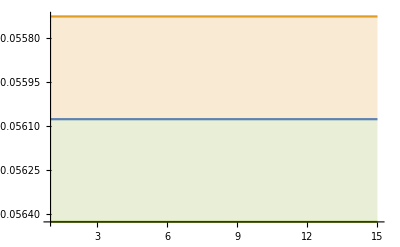

```mathematica
Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,15},Filling->{3->{1},2->{1}}]
```

```mathematica
SpoilHWFLOPlotN3=Show[Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,Length[meanErr2[[4]]]},Filling->{3->{1},2->{1}},PlotRange->{-.15,0}],ListPlot[{Table[{τSteps[[1,i]],meanErr2[[1,i]]},{i,1,Length[meanErr2[[1]]]}],Table[{τSteps[[2,i]],meanErr2[[2,i]]},{i,1,Length[meanErr2[[2]]]}],Table[{τSteps[[3,i]],meanErr2[[3,i]]},{i,1,Length[meanErr2[[3]]]}],Table[{τSteps[[4,i]],meanErr2[[4,i]]},{i,1,Length[meanErr2[[4]]]}],Table[{τSteps[[5,i]],meanErr2[[5,i]]},{i,1,Length[meanErr2[[5]]]}]},PlotRange->{-.03,-0.005},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]],markerlist[[4]],markerlist[[5]]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]},PlotStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau_{\\text{steps}}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3(\\text{NLO})",Magnification->1.2]]
```

-Graphics-

#### QCD mNLO - gauss

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={380,380,380,380,380};
NWalkers=200;
Nf4α1LoopBig={0.229421,0.229421,0.229421,0.229421,0.229421};
aList={1,2,3,4,5};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
csvData=Table[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"],{xx,1,Length[aList]}]
```

({mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.0693947395561387, -0.06996588646675794, -0.07033506461873527, -0.07565316998249012, -0.07327531138337844, -0.08131973542563894, -0.0743761285085898, -0.08221289900466339, -0.0892170402449708, -0.07261104397125728, -0.07596160415119808, -0.0769448420391358, -0.06736217033226037, -0.0673009046046662, -0.06759695721041095, -0.06871737928653705, -0.06877071562389699, -0.0688142822977844, -0.07255106285042712, -0.11955912004138637, -0.07084126272247245, -0.06817664826446056, -0.07032839809797349, -0.06790812152801964, -0.06505814245099369, -0.06243991164040177, -0.0642157038457341, -0.06127534839199538, -0.061444216691796345, -0.0631958821315079, -0.06277004653270382, -0.06546822508480593, -0.06610150774581364, -0.06696979509055438, -0.06644870585127831, -0.06316933633076521, -0.06140888755669551, -0.06473171527420313, -0.06480518900182632, -0.06643309327300502, -0.06889075935768742, -0.07622288194167484, -0.09921713361694609, -0.06433812330002862, -0.06896266692258668, -0.06389385470844731, -0.06508499831663085, -0.06807102359233728, -0.07087501614010633, -0.06670393026265281, -0.06486835819539036, -0.06698284634353004, -0.06453176695432473, -0.06784721617315448, -0.067321974472868, -0.06732456114575656, -0.06697569412942901, -0.07387307015035183, -0.08599973332090023, -0.11948958155934672, -0.0818434076707236, -0.08082458389915563, -0.14379546317121192, -0.07278840225284441, -0.0702766104617821, -0.07334113794150075, -0.08779136431608126, -0.07630771500027754, -0.07527020209053553, -0.06880773804513014, -0.07024461497442727, -0.07589684048545997, -0.07223134399740247, -0.07240654749096655, -0.0723099786252942, -0.07385613426959113, -0.07188129685980277, -0.06987800773948151, -0.07408963258371107, -0.07343995570516114, -0.07314105989158698, -0.07743016303250061, -0.07210259517315737, -0.07193167437076085, -0.07169536122177017, -0.07363115914969773, -0.07170262588220244, -0.07235174838765743, -0.07974486144503792, -0.07044267558092017, -0.07778296239854725, -0.07820419252922031, -0.08926017746807269, -0.08961535834455546, -0.09245483487140628, -0.10274538549138829, -0.11749471625193511, -0.15768698458541364, -0.09616822058300892, -0.10039249556660386, -0.08444526930373752, -0.09545478509995661, -0.10592222537553145, -0.12989921367076426, -0.0956497090684193, -0.08842168750382255, -0.08583373555534259, -0.0872111501867729, -0.08722749281323298, -0.08371558489674029, -0.08165828026365365, -0.07675264870228671, -0.07486679720858966, -0.0725952428696142, -0.06898265603790724, -0.07030386596856296, -0.06965969336695504, -0.07519759991598572, -0.0715124997995891, -0.06949169732374964, -0.06539942493871394, -0.06683759711487484, -0.06705596907737908, -0.0631868041572212, -0.0640096497658082, -0.062398468036706234, -0.06088876594960019, -0.06071500049664465, -0.06317258087387728, -0.06821680215373832, -0.07017927211994446, -0.06893982222029629, -0.0717712040044695, -0.07496598052626667, -0.0747762491717671, -0.07478108249567933, -0.07684600966042067, -0.08168079304181568, -0.0902531506719244, -0.09349313105994778, -0.08438983351075323, -0.09552325003528869, -0.09566645432794851, -0.09143683660539556, -0.12070682182868364, -0.1118967614310158, -0.1249410865386779, -0.08876141566342004, -0.08449805146836085, -0.08495439244373737, -0.08313460592387649, -0.07978233080392086, -0.0947827994951737, -0.12982860170349375, -0.0892216384984361, -0.08503501868066615, -0.075631499500693, -0.09111739942711973, -0.2099103737345732, -0.14444132642961902, -0.13781418646359772, -0.09415505772075199, -0.08635320041477836, -0.07946113711974123, -0.07704094527204633, -0.08246543355699522, -0.07450778041917812, -0.07409598580945832, -0.07425583859395725, -0.08415536496721882, -0.07940706524745654, -0.07647338219478117, -0.0701122533996584, -0.07232530367237817, -0.08408405227740505, -0.11299484720601845, -0.0830134218373049, -0.08846675587643037, -0.07353539988428766, -0.07774402265756626, -0.08137880441399802, -0.09443835027350406, -0.07771903756580349, -0.0828042941441187, -0.07429990811210632, -0.07679783781593442, -0.07740674701147798, -0.07232124463806891, -0.07056177534601747, -0.06837810845834195, -0.06759441507237227, -0.06756777452726002, -0.07765866610426773, -0.07551647592252156, -0.0728834309067445, -0.07995188305398834, -0.08988707223046816, -0.09026959106603023, -0.10404795549423203, -0.10126981170970144, -0.0963661209443771, -0.09530966499707842, -0.09463678565561501, -0.07888644645262659, -0.08443424383874419, -0.08750583517778743, -0.0788749722072412, -0.0799157992033654, -0.07256794241834838, -0.08372925922176287, -0.10287478962358132, -0.13259673640936365, -0.10318992172217376, -0.07490495143335754, -0.09494907874748316, -0.09055656748261587, -0.09451338447592365, -0.08148121227097194, -0.07729613617991415, -0.0752729685814645, -0.07781075750622302, -0.08281967308690656, -0.08734571385686365, -0.11135732641585662, -0.09407099692141947, -0.17635546234743724, -0.11381205797926365, -0.08829088544777558, -0.08878140946861426, -0.1033612858495049, -0.08559399035161111, -0.07966217553764991, -0.08501944862095173, -0.07970796849020587, -0.07993794123553183, -0.07716722849974687, -0.08584631896939338, -0.08337771685516084, -0.0895739410790476, -0.08579438454141719, -0.08089880260062213, -0.07471912553508915, -0.0814696815344281, -0.11391293116014639, -0.11036235252094427, -0.08739869717083601, -0.07325343132183083, -0.07505618668519158, -0.08143965522113368, -0.07661185342152699, -0.0725877035541685, -0.07798726935643728, -0.0803532934056162, -0.08152460337220667, -0.0800144003166214, -0.08840646950590109, -0.09461269529100874, -0.10293438266548609, -0.08880213958993478, -0.078640790223373, -0.08610818817753767, -0.11330861770583371, -0.0989788333244805, -0.06934605292937503, -0.07159223236714976, -0.07290111249327794, -0.07642426750573149, -0.0772029105281528, -0.07598438967685886, -0.07486845920397472, -0.0675353124499481, -0.06532548551895989, -0.062208369877372945, -0.06444266966833656, -0.0616930419490326, -0.057814691756427616, -0.06530636786465843, -0.057276799122320025, -0.055591578708025446, -0.05897445560571469, -0.05557672106858356, -0.054440213515994755, -0.05687486082345834, -0.05732738055425933, -0.058257379379416524, -0.06138344465985977, -0.06822616623768495, -0.07386756797130402, -0.08471849227904998, -0.0695045183146145, -0.0734722346780296, -0.06823657310556877, -0.0675719986284694, -0.07383767334649119, -0.06629992424448827, -0.06368160967690681, -0.05908932458666903, -0.062234103197366795, -0.06421369121177947, -0.06522812217702961, -0.06304618015835621, -0.060613732133684046, -0.0630128011472819, -0.06832728328089574, -0.0632596044632009, -0.06737025820824731, -0.06672872108494578, -0.06922842468083286, -0.07208885651316489, -0.0732501788889601, -0.0745904982938629, -0.07982352382960045, -0.07912804530608378, -0.07284308211052391, -0.06685058627799284, -0.07290454744124208, -0.08592661186573396, -0.09114208877205701, -0.09154342012435447, -0.09197879945710019, -0.0815336304144211, -0.11668603847343718, -0.27243413969282115, -0.4061798345110355, -0.2827049966780141, -0.1412132279322733, -0.36358038215216154, -0.14095550071186266, -0.11234685601800634, -0.09597374502812221, -0.09426224951753505, -0.10891285306895496, -0.14828779772532125, -0.1961353132994146, -0.23795532278355447, -0.8167008642566612, -0.46663590227233126, -0.1566356719038989, -0.1294545526686106, -0.143186663124442, -0.1739256212278285, -0.14853814409132818],[0.0034290114965377944, 0.0035171963877706747, 0.0033593788705462545, 0.005329437955347094, 0.005317681420356127, 0.012017344789084075, 0.0060452095698717906, 0.014949068951962585, 0.02510510872341249, 0.007596732514742507, 0.009553755711327747, 0.011042041987793306, 0.0030983363933535105, 0.003628250264009353, 0.00388063622076085, 0.004102079068103107, 0.0036104655606140974, 0.0037312235470472062, 0.0055999015635507365, 0.049537807114312535, 0.005513626254250495, 0.003980790986919323, 0.005188945855781484, 0.004860017859294165, 0.0038187293542366178, 0.0031947013539021297, 0.003697926303620438, 0.002722960331653968, 0.0024685233111204755, 0.0029543883691960466, 0.0023514547933709035, 0.003542667187112878, 0.003940572530413207, 0.005163184434829957, 0.004024279352512538, 0.003120345552328769, 0.0033449611378841104, 0.004832665909599896, 0.004856420516770682, 0.004477357682726043, 0.007164190789952587, 0.013758829523112227, 0.0381481920829283, 0.004770187967445228, 0.00819191664896138, 0.004256557594838454, 0.006054899057142689, 0.005597297098911814, 0.008571629807529313, 0.0051991956687343355, 0.004170568347596762, 0.0066349492324466325, 0.004137894001542915, 0.004832095127420026, 0.0046514244962773165, 0.004579111808561342, 0.004225640867265183, 0.011196703874459724, 0.016536589339882665, 0.04501576478629811, 0.016733187155581603, 0.017551260132791503, 0.078703768347504, 0.008789745259113127, 0.0070002801064422285, 0.008841458031553794, 0.02152383153193721, 0.01218560515337957, 0.009479742074084033, 0.005332980505231993, 0.00562783302096771, 0.007855105894857316, 0.0062283391748685175, 0.006469518712235389, 0.004326924000845075, 0.005959765810333615, 0.0050348966173338035, 0.00453579593049894, 0.008475148012490743, 0.007999060339582283, 0.0066070072307958415, 0.007366226214710555, 0.005539261577974951, 0.005229777118962413, 0.005369244508521431, 0.007934937615630806, 0.005690190771255615, 0.006287895238627471, 0.010132096559675476, 0.004794278632826708, 0.00963996949665448, 0.007797373530028995, 0.012466606234096568, 0.012681158709301673, 0.015552773134597523, 0.021769258681422213, 0.029631162506376967, 0.07102988723653293, 0.01417607460519489, 0.02208578018898496, 0.010870135922393828, 0.015938175786173573, 0.020210175187560853, 0.04754290359881401, 0.012982564008173181, 0.008970862187983078, 0.010354060864986615, 0.010474086631839906, 0.014384486114466341, 0.00877838234756325, 0.007848746882525718, 0.006239863011463423, 0.0060823985827130915, 0.007281915580704574, 0.005449658428805809, 0.006059280607843626, 0.005553110417802604, 0.006859129741954561, 0.006782390758330301, 0.005452420946867101, 0.004065357580735857, 0.0041548055579774, 0.004090377234757937, 0.0032317774988991623, 0.002921539798195196, 0.002718832675845941, 0.0029826508980242386, 0.002911492661200419, 0.0035524268731490435, 0.005382631119768798, 0.005612482992172905, 0.004779549043900782, 0.006490710693994972, 0.006715657381414175, 0.004650203729700843, 0.004726377763315386, 0.006797198520767639, 0.009199338884822366, 0.016065801397810008, 0.02028926671304724, 0.009886044889417174, 0.013707584287413943, 0.016845591023436433, 0.01573714866160638, 0.03164478473269351, 0.023789816362750904, 0.04145006561547647, 0.016290003481973705, 0.012283316975465062, 0.013897750634464249, 0.012030955535763591, 0.008613194181459012, 0.021582769724766148, 0.05196202387663675, 0.018879962918840493, 0.012189805812406083, 0.007173956987132732, 0.01764279618253813, 0.11174789374956101, 0.05852287899613827, 0.05175453102281341, 0.01854838859992333, 0.012135012509800007, 0.007001784532308226, 0.00534287450673366, 0.00776618877054336, 0.004916990859059798, 0.004821433328698704, 0.006067243498375533, 0.010288563436831263, 0.007391683298996952, 0.006254998931826374, 0.003904473247536208, 0.004683752478842471, 0.010472901359278195, 0.03442852944522057, 0.011771485285164033, 0.019193089157407237, 0.005671810958810765, 0.007335031318060543, 0.00733941866647172, 0.016553458585744325, 0.006838017049327504, 0.011470762081621896, 0.007662329467540954, 0.008719070187114502, 0.006122670093800414, 0.004705529964061658, 0.006658849484027886, 0.005780809433494017, 0.0030589253173911577, 0.0029802591998037264, 0.008507931817412984, 0.005119515179330011, 0.004123832728823191, 0.007713778965013946, 0.015352099566010684, 0.014157919087275884, 0.021456288809797577, 0.014576083026794143, 0.012793989807429304, 0.012350109274599954, 0.010671912145153553, 0.0057287631499594585, 0.008545337281239207, 0.009158569301379704, 0.005273057975330086, 0.005463706336566489, 0.005234279022320178, 0.008954078027354219, 0.019015436831875315, 0.04292336511834711, 0.02170559896777375, 0.005674680821545489, 0.017218429158293656, 0.012710377902732621, 0.018899112439323313, 0.009976973987389908, 0.005315759033228456, 0.008517686372416802, 0.008127708531354222, 0.012363514347119893, 0.020682698446260354, 0.041448426054928315, 0.014208198118127664, 0.10328601404507333, 0.02631659094089023, 0.013195712387148813, 0.012037695080616998, 0.027055269754185256, 0.013368290620544006, 0.01319554453271749, 0.019241941658542948, 0.013484439744470568, 0.01533476548869148, 0.012662074154581975, 0.019220617630103052, 0.016413351994908974, 0.0253178502962659, 0.02469397890125047, 0.019999760404190724, 0.011585552594922862, 0.010850027140890487, 0.045070865992142994, 0.04472389205451725, 0.021593105748951884, 0.008211921203446965, 0.00940687585199863, 0.013423905896953716, 0.011725979483740757, 0.009556362102245978, 0.014547342822281872, 0.016567785193267372, 0.015983894350933607, 0.012514547484469568, 0.01609844188149119, 0.01887737481817423, 0.029425403438602775, 0.01567012196125262, 0.009523996037727637, 0.015817359719199047, 0.054322091053119304, 0.042035872123292614, 0.010155884168346401, 0.008377279173382728, 0.009213909334626553, 0.010118271681628424, 0.009637108436563046, 0.011083859253631792, 0.01367969911886779, 0.007045236962417434, 0.005428552780569544, 0.005806479998885186, 0.006416313742516942, 0.004025188391892024, 0.003339637346926585, 0.01148477438844341, 0.004655366571406985, 0.003537432175255932, 0.006324895832106487, 0.003597595633362317, 0.002884152574885095, 0.0036317131428445846, 0.0017077850575175225, 0.0022690412876109883, 0.002981461454593472, 0.007305706622476102, 0.007834414426912276, 0.017563102002655373, 0.005274807658237991, 0.008667795889133542, 0.006007810259442085, 0.006067226898158464, 0.008980617805692544, 0.0044576791428546, 0.004140729419658104, 0.0031911481284812525, 0.00377393061995488, 0.004405256605845886, 0.005984607334249026, 0.006023123797704441, 0.0034130839146891035, 0.0038285107373558537, 0.004703775976573697, 0.002935993249338031, 0.00404259339386357, 0.004152357541931533, 0.005705905942300643, 0.008330532549831375, 0.009146644100962964, 0.009025820993686772, 0.01048551335178057, 0.011054407553544525, 0.008611619702712259, 0.004292686292650063, 0.006389080547836714, 0.014973569786220744, 0.0159036036528199, 0.01608712179778554, 0.0181620902422899, 0.010719515624018572, 0.03497892951257971, 0.15053939768118332, 0.24037905944769425, 0.14619525414796047, 0.04822276145615923, 0.19135367506505988, 0.04597249222116821, 0.027182912600414205, 0.016237898041560832, 0.015381270554844765, 0.0208765733628533, 0.04129493591735439, 0.07352662431874919, 0.08096968944428583, 0.42228358036604974, 0.22664063126169362, 0.04454245043083631, 0.02973912305106724, 0.03171759190274695, 0.04924802260609665, 0.03230607462374276],-0.0659411,0.000423279,0.802478}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.05553655202087442, -0.053835943202518506, -0.05410177944748117, -0.056211570473684636, -0.05576112051353504, -0.05520597612081169, -0.05526507375701913, -0.05664398703976422, -0.05627019338806924, -0.05729366179969094, -0.0576809302907872, -0.06007757967919464, -0.062119516011595925, -0.05893572523391304, -0.06014550270022944, -0.05798503499489542, -0.05804048567233297, -0.05852832828296052, -0.06019996419229525, -0.06256499710764754, -0.06276084895255166, -0.06374180127312144, -0.05730594683145531, -0.05802780114365008, -0.05751999607673442, -0.05660999157326108, -0.057033751639171515, -0.05469052586957423, -0.05499384556716868, -0.05478714045313579, -0.05614999866771918, -0.05669619622371235, -0.0567311096277226, -0.05899434299138986, -0.05548368580679161, -0.05452412244115166, -0.05580512720904718, -0.05546366132960239, -0.05698555343362487, -0.056713966799509984, -0.055816248916307314, -0.05682216369502211, -0.056142950929881315, -0.059196619507216795, -0.0582839595804849, -0.06076178277765265, -0.06542790432186447, -0.06598718458161354, -0.08139415826293268, -0.06308319388166243, -0.058582581765470265, -0.058073500243579136, -0.05764526635349222, -0.05969668687303529, -0.060710685022572854, -0.05967259812164944, -0.055304588465896067, -0.05456035016669809, -0.05565347864567486, -0.053402173000135014, -0.052658092116033756, -0.05233784709410338, -0.05404414230260405, -0.05329357886216123, -0.053248675577040896, -0.05290838496930481, -0.05324791094700087, -0.054774457355106276, -0.053729684297663304, -0.05393939049451425, -0.055523149997401745, -0.05549309727053929, -0.05415574872464728, -0.053852269490599854, -0.05387932704925503, -0.05415102492309374, -0.05410733133333045, -0.053520830231746905, -0.05248637254819798, -0.051120659067575625, -0.052678014119847794, -0.05454218441474901, -0.053377430233739705, -0.053721581669708994, -0.05479772294841304, -0.05438386073077602, -0.05461710682189136, -0.05583484315000389, -0.05793049964246686, -0.05792079650905917, -0.058820906000399256, -0.057670194587857215, -0.057898133598761496, -0.05763724674192135, -0.056893889219977456, -0.05832207297128129, -0.060357582917666214, -0.06176778988902977, -0.06721682161809879, -0.07122783487298179, -0.0695937430523363, -0.0736113020713717, -0.08515152669413675, -0.08453941592385911, -0.09044475983954252, -0.07709394593991677, -0.08975093979817207, -0.07449897597000746, -0.06941362344237481, -0.0677775653431712, -0.06996066210716088, -0.06818698067092598, -0.07039601264285061, -0.07077668658222695, -0.06802502342347483, -0.06508078339002964, -0.061527144923271056, -0.06094001646110364, -0.06096112989681317, -0.05944518080207295, -0.05704614940342251, -0.0587793329355985, -0.059076733766669165, -0.05957568663062039, -0.06215071095568191, -0.06035421071005944, -0.061083562387901705, -0.061271481922016834, -0.06404761612597905, -0.06645594355048197, -0.07002276195032837, -0.06267400416665173, -0.06353288859499036, -0.06598058093113252, -0.06619168090444977, -0.06287205471187812, -0.06138594467204104, -0.05891175546085616, -0.05857647681753086, -0.060682091896094845, -0.05941499929176799, -0.06344920806745208, -0.059700843730782334, -0.06111504421729624, -0.05882768382185558, -0.0567544276963036, -0.05453841849466981, -0.056827988940217296, -0.05808543678859322, -0.059709290449813546, -0.058771829279375624, -0.05916664955984619, -0.06086611023336645, -0.05852344330853804, -0.05823627257483662, -0.0592345669777738, -0.05985028969386513, -0.06117611460201702, -0.06039313276020359, -0.06046145316069819, -0.06010273287198951, -0.06051319192111364, -0.06294376330583039, -0.06370911014088007, -0.06642845231443827, -0.06522748234822194, -0.06415374599000524, -0.07132069154656444, -0.06733934536325119, -0.06824406810387575, -0.06551603187815642, -0.06860786463687887, -0.06309400047766561, -0.06272954983098715, -0.064360448680561, -0.06391612599274174, -0.06491972429590917, -0.0677718801883292, -0.07038492524151906, -0.06690906223065703, -0.06605497662816763, -0.06425362435033656, -0.06514911891042148, -0.06330880345590363, -0.06420232749820146, -0.0630498927809276, -0.060247085856860144, -0.06016630873375355, -0.06066234817665932, -0.062381457647367224, -0.05843151655268147, -0.05839714545525787, -0.05851950276303822, -0.056683162911152704, -0.055672194804620295, -0.053806175126563806, -0.053115394488593655, -0.053520128461798114, -0.05405518334812336, -0.05370041431965556, -0.0540705044329697, -0.05318394935529876, -0.05224148164510922, -0.053047810855631296, -0.052269039264190825, -0.051834034958017736, -0.05331281016171711, -0.05264560800975876, -0.051791465509464084, -0.05112380644508973, -0.050631741640640514, -0.051643933879226264, -0.053373515460136814, -0.05274623923486769, -0.05084945341799951, -0.05034049670881742, -0.04988785763018298, -0.05016104136174035, -0.05034081867761815, -0.05032376791731096, -0.05140329518761328, -0.05386141394992471, -0.05272024854026541, -0.051381211291016325, -0.05347496525116473, -0.05566876704780054, -0.0537517780703494, -0.0521488306356408, -0.05265915975359513, -0.05308929610912172, -0.051397665673519784, -0.0496421058301087, -0.05068545455567609, -0.04993719701895615, -0.05121956519747235, -0.05122054958086551, -0.05089050924777028, -0.0521871075336785, -0.053008717200017895, -0.0546152265824812, -0.05172582614424553, -0.05413872260113331, -0.05598529479176105, -0.06733249917343707, -0.05919386863536538, -0.06687125471342042, -0.05828312863577329, -0.07372140211392572, -0.08102054457628899, -0.06940365396521112, -0.05988627186119981, -0.05926352699582891, -0.05930129846547053, -0.06215212332666797, -0.06574670086396114, -0.06901480609244233, -0.06526351252139669, -0.0619693786662475, -0.06172143619535379, -0.06103483208890613, -0.060698783205795456, -0.06458557602797343, -0.061529154713190926, -0.05951751022545411, -0.05830047593606879, -0.06071848751790381, -0.058240706153228926, -0.0611897395067241, -0.060191987811901146, -0.05784243152918258, -0.058504794569714406, -0.06097481240367036, -0.0557346491802899, -0.05550908505308234, -0.05695765608971371, -0.052497506224260596, -0.05351695510839024, -0.052119286417291785, -0.05402464601545177, -0.05292177109724642, -0.05342896971980307, -0.05213401286233796, -0.05117626787726808, -0.05070043804917398, -0.05110888013236747, -0.051984016044901535, -0.05394238148370245, -0.05711610546467887, -0.05503560885920075, -0.05441994235728236, -0.05502499378266516, -0.05357880093815607, -0.0538621028258487, -0.05570855588952486, -0.05755451689586058, -0.060910524501392595, -0.062317078832646776, -0.06318563398641087, -0.06440772838283099, -0.06404261850991622, -0.06143619095737556, -0.06145310778044085, -0.06064103144168478, -0.06217730998437128, -0.06279600696976327, -0.06347682252938701, -0.06330653273409306, -0.06763140024611068, -0.06614028033982267, -0.06065729877766089, -0.06291922589435553, -0.06208890268059928, -0.059990686541108354, -0.057916606772406835, -0.05607790205380167, -0.05626198554261979, -0.05985099859623095, -0.061588104125007634, -0.05802509503408912, -0.05731473858094311, -0.06277450329069123, -0.06687809709089927, -0.06842927287600027, -0.07832273380874025, -0.07884925422912793, -0.07004359626969132, -0.06945981448469876, -0.06624586115876172, -0.06478161628298154, -0.06036638050793618, -0.06069483021265724, -0.06315415437419043, -0.06398470234005466, -0.06498525258559716, -0.06962487045538486, -0.07180715503184835, -0.0784781981979085, -0.06350118656323929, -0.06460268298105806, -0.0624831805088841, -0.062148200042452695, -0.057489277754555784],[0.004624062008180376, 0.0035553783819632207, 0.0036443795506713294, 0.004221404300256223, 0.004120406007759979, 0.003712341630340059, 0.00354075231705132, 0.004069167334369295, 0.004029610810023173, 0.004401626647779867, 0.003835839691863206, 0.005025046574883135, 0.007452051036236369, 0.005195606670974684, 0.006174552980658109, 0.004323044750110602, 0.004334905101571252, 0.004538681424327772, 0.005551964901435608, 0.0065126536687449025, 0.006484971181788063, 0.006890154344148699, 0.004381140855334155, 0.004689427260223942, 0.004398768769970442, 0.00425079674600129, 0.004358406765437827, 0.00372918860154623, 0.004199138062167706, 0.004205712738869693, 0.004330042088258524, 0.0049710907809128275, 0.004919830066566431, 0.006536841638430733, 0.004445243009019417, 0.0039015932819406875, 0.004657908500761675, 0.004003964538418038, 0.0050750717467382515, 0.004656517345658867, 0.0041956872194721, 0.00464499386776744, 0.005088240927294974, 0.006484828135646219, 0.005278136214639386, 0.0074326977157599386, 0.010724794109523428, 0.010501751805585024, 0.02424497427181509, 0.008570096345010127, 0.006311154154797507, 0.006083514932088514, 0.0066176245838043025, 0.0073512121518724185, 0.007765432937778887, 0.006445498595181387, 0.0034901024645088634, 0.0034214824954942155, 0.003761599303471088, 0.003330721110141352, 0.0028894984219856065, 0.0027363406580333217, 0.003372368774814702, 0.002621512569901211, 0.0026074587904433635, 0.002668364457405223, 0.0031918806509322333, 0.0036638079848710587, 0.002901393567116382, 0.002950408242846769, 0.004038595017520919, 0.004006987093383896, 0.0031795391980615957, 0.003058537781388889, 0.0027753039371848313, 0.0029676146040033668, 0.003201059259303814, 0.003073059138245591, 0.0027313613055109996, 0.0024050736538802036, 0.002887415849903573, 0.0032735636446599077, 0.002941971477799581, 0.003066046744717127, 0.003722177761837922, 0.003476256624085238, 0.0034784293979548573, 0.0043427292083356534, 0.004981160584436135, 0.0050364170227271444, 0.005713909995664773, 0.005096011230137119, 0.004989376056928642, 0.0050165243149674545, 0.004781266107824947, 0.005745697531479163, 0.00654318069301992, 0.00710563424510645, 0.009146465298834124, 0.011624508604033457, 0.010615915779607672, 0.012009712996832613, 0.021781071208140275, 0.020821158122482003, 0.02373117580963312, 0.014782608942426865, 0.025840512790261217, 0.012144112701572587, 0.00887730896610498, 0.00732341073011208, 0.009900328378823028, 0.00905239338050048, 0.010402004095556411, 0.010120852393442315, 0.009303268507907619, 0.007436598017465377, 0.005268102715205049, 0.004785391210792321, 0.004764353665680267, 0.0037879588977357726, 0.0030697833631435, 0.0034850617088808492, 0.0036440473558460263, 0.004051834366363894, 0.00505426048890676, 0.00425082363825382, 0.0046451164808431235, 0.005360847918749931, 0.007094949707406021, 0.00864263578128169, 0.00981309672105651, 0.005596845419833424, 0.005446725211231764, 0.006088249962270735, 0.00661969773634074, 0.005257773816383844, 0.004715366354338531, 0.004946535199188198, 0.004847892212404928, 0.005322192822160771, 0.005239854976251396, 0.007555270670928346, 0.004537859458639238, 0.004793785129853708, 0.0037189509325584484, 0.002758652289098296, 0.002301992513154708, 0.0027588416779336378, 0.0035266474262790194, 0.0033804124438010456, 0.003258268523886014, 0.0032806207387456616, 0.004283055866206954, 0.003965613366233235, 0.0033878831774548984, 0.00389119666834854, 0.003936747022194201, 0.004351468145879319, 0.004202089125777555, 0.004920441076084018, 0.004328364201392368, 0.004009070514890966, 0.004107844454894541, 0.004032357333125386, 0.005139289126575778, 0.005503880922593185, 0.005052329936985043, 0.010166989962156469, 0.006444702609631948, 0.008112075990564883, 0.005919653665261587, 0.008073647073892753, 0.005166244387053426, 0.004754755459547214, 0.005296833820239333, 0.005461355217857182, 0.005454197244511711, 0.006549983031428805, 0.0071294188758443885, 0.006028328430781209, 0.006058248688401158, 0.0053906195883208765, 0.0064410851732871225, 0.004912000785763578, 0.0052936650423262375, 0.006122588235158649, 0.00464428547000379, 0.004510657649141661, 0.006122338130645386, 0.008161782236285943, 0.006400579843607691, 0.005765122387499754, 0.0054893636819357125, 0.0043627089614933666, 0.005111730708039486, 0.004122132335123829, 0.003053995004860847, 0.0035414892183431666, 0.0035789306053552574, 0.003479481862243343, 0.0032418348418269674, 0.0029394214646359944, 0.0028815296435027917, 0.0029451183076785238, 0.002642030132223755, 0.0029257472807307254, 0.0034941590045784007, 0.002901672829518045, 0.0026968804318480027, 0.0032504344438544466, 0.003020539383513193, 0.003662658466831399, 0.004867978815649929, 0.004613373737293542, 0.0033562879432696945, 0.0033953739655237227, 0.0033483173912733644, 0.0034987966256265495, 0.003670102957469829, 0.004261505874927007, 0.004534259420819345, 0.005610338259624392, 0.005051566797050165, 0.004653719510237239, 0.00569079472750143, 0.007091267183484898, 0.005558808985785406, 0.004588357465902274, 0.004953419560786091, 0.005097665532596794, 0.004704334779617101, 0.003939645811970964, 0.0044094747573619605, 0.004034030496206536, 0.004591612887496859, 0.00486054918914716, 0.0046054838260942265, 0.004337134759181055, 0.004575181679964312, 0.006229052725387229, 0.004532544981441244, 0.006201144333660981, 0.008472482574042074, 0.01933464850405034, 0.011084147316735295, 0.018383150968645526, 0.009990320439487837, 0.024753439954914774, 0.030271980308177723, 0.019175360075514736, 0.010798611378259899, 0.009121618608436998, 0.008291803011582883, 0.009394101284061936, 0.010845629626267886, 0.013664194938721343, 0.010087587109613695, 0.00781561535618088, 0.007934117501153568, 0.007845620095388493, 0.006916045267012046, 0.010202874116114024, 0.008170280419438217, 0.007902845640527137, 0.0065555030312721895, 0.00785745029206204, 0.00629520264629434, 0.007471695526874002, 0.006636662146743066, 0.005774074555685886, 0.006327122712022647, 0.008274693440605965, 0.0049719423067770266, 0.004918221462217439, 0.005942037246942432, 0.003924726228874228, 0.004573556160424013, 0.003690258913387958, 0.0038819567487307183, 0.0035504854770720433, 0.0038517285621794146, 0.003771584394162351, 0.003645903030548666, 0.0035541751171462143, 0.0037348120995486273, 0.00414257480928507, 0.005507231479586987, 0.006883467193802824, 0.006281995881970495, 0.005190806060219415, 0.0055593176649767215, 0.005027623936129451, 0.005202873905356272, 0.006485456975414839, 0.006987594557393391, 0.008765844572486525, 0.008880486635980728, 0.00993403577945764, 0.010712435351668242, 0.009264774583161852, 0.0076005267754586485, 0.0074104904435522674, 0.007616444810119544, 0.008404559533717167, 0.00899432014254596, 0.008003356532218536, 0.007705046810003059, 0.010238997448591983, 0.009038650181859391, 0.0060740869360235315, 0.0076106993248248435, 0.007221952738651911, 0.006201556796367748, 0.005011707417510639, 0.004251654432455462, 0.0040896369360973696, 0.006470047992080726, 0.007122420264332999, 0.005531379073296793, 0.006499746017456654, 0.011299401498502698, 0.014642585489510963, 0.014928722461740667, 0.02127741671548243, 0.021682602249882235, 0.014212941852759543, 0.013158539429945099, 0.010485256554319417, 0.01013407642732159, 0.00749761370453597, 0.007858648074061803, 0.009414075576446988, 0.009807980390217068, 0.010079312310592259, 0.013704484906644, 0.015683456168998224, 0.0205625811296971, 0.008697236595896968, 0.009814966870357041, 0.008142592651146117, 0.008253306391374955, 0.006368063732925886],-0.0505206,0.000794035,0.28901}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.03384381044711053, -0.03415197087628393, -0.034482781146147494, -0.03452901907392177, -0.03539950603114207, -0.03509446579366751, -0.037485298488287126, -0.037777531390006676, -0.03730744354530854, -0.037824194491638534, -0.03677236748198627, -0.03602910787426745, -0.035937413925604164, -0.035361856221622516, -0.035167806173533, -0.034671583258759436, -0.03431456400121249, -0.03443800302322061, -0.034616073877764005, -0.034657870398451224, -0.03479175443882647, -0.03464517116471621, -0.034936093406174366, -0.03500575049666925, -0.034693434687286626, -0.03446226600842443, -0.03456629370207651, -0.03446638033207402, -0.03429948245590236, -0.034416061814336374, -0.03447832711860629, -0.03461501403342425, -0.035141913024030254, -0.0353722191478424, -0.0357163979909858, -0.03583717366678936, -0.03590835577781835, -0.03629758823580022, -0.03627890991693916, -0.03626169476947624, -0.036433969700521984, -0.035615452839970946, -0.035794107774759984, -0.03617083779246512, -0.035913055518264604, -0.036667483487883894, -0.036113550137587616, -0.03568709293827487, -0.03641213776869434, -0.03644580476939333, -0.037057704917466516, -0.03695874705962684, -0.037075737227421704, -0.0373663586085114, -0.0370762702461421, -0.037667949841252026, -0.03733970192296862, -0.03726861625309496, -0.03772165548859356, -0.037838322134226006, -0.03726744506626148, -0.03696725553036077, -0.03709152143512827, -0.03743832515816479, -0.037616850783108065, -0.03757263392927919, -0.03733807338783632, -0.03764724146257536, -0.038412149607560064, -0.038582519635419844, -0.03850594545831414, -0.03868065288243763, -0.039014249262912394, -0.04011022917936678, -0.04153753167343178, -0.04070548881987457, -0.04016318559234176, -0.04070712955408506, -0.040201474707112654, -0.03984942730443247, -0.040392306869688234, -0.04026684915230441, -0.039983791340631986, -0.03998314829217338, -0.04022292540969223, -0.039924012730797015, -0.03997290659741376, -0.03999297727812292, -0.03915176040748781, -0.03938105297561504, -0.03998394696072267, -0.04035301328050419, -0.03989622998726655, -0.040774630579149276, -0.03998190566952074, -0.04043107404840689, -0.041000996422534706, -0.041060346679751156, -0.04111210609171452, -0.04043214125242494, -0.04109404923063167, -0.04190992656616816, -0.041921977270910044, -0.04336365798842068, -0.043546886016540824, -0.04238514921386409, -0.042309681391852975, -0.04128705329959728, -0.040440982242415234, -0.04017879590692553, -0.04014256168068678, -0.04032725931057474, -0.0413397776612357, -0.04150174616378776, -0.042395942725347434, -0.04300975620243788, -0.04245494812472294, -0.04185794713621676, -0.04185771601046033, -0.04236394213568274, -0.04193761882653484, -0.04283483819788399, -0.04333615277046516, -0.043556739528540174, -0.043887149828351533, -0.04369230037694938, -0.04315088140056744, -0.043562480300232104, -0.04410604309371811, -0.04428890247249033, -0.04477324358764804, -0.045742004574725624, -0.04718154963631787, -0.04781526832132855, -0.04788386416238368, -0.047810309971851844, -0.04822632856880636, -0.047731835727859356, -0.049117027522931525, -0.0496851085017874, -0.049331528214772276, -0.05024452632317042, -0.05204632956083656, -0.052362062157376994, -0.05015241761608221, -0.05146499698747574, -0.049083434035039064, -0.04939578951013924, -0.0482407568424056, -0.04895353422918937, -0.04777148614949422, -0.05086046810549785, -0.0512499795373578, -0.05213222654885032, -0.049271141414577516, -0.04991735056102226, -0.05054763394000371, -0.0511176277948787, -0.055169231118245586, -0.05092887972574335, -0.0479857902863825, -0.04795877146394122, -0.0493372034126752, -0.04951075613419958, -0.052233399435528655, -0.05155506393753769, -0.0520279619966132, -0.049051205833502025, -0.04960851450143938, -0.049292685643937406, -0.0509322068718911, -0.050291676224949004, -0.04875025120309518, -0.04717955524213661, -0.047839749913749896, -0.04607782407105948, -0.04636537803830611, -0.04721785876676264, -0.046887589067523376, -0.04749258735806315, -0.046430108188947196, -0.04640375953989325, -0.046607624502971214, -0.04571780735912839, -0.04543080170833724, -0.046561765453451455, -0.04736083048730604, -0.047066130721289325, -0.04595731668952915, -0.04685349793449559, -0.04674448533822554, -0.04666159463184857, -0.046944512988497215, -0.047009239713146994, -0.04606966053810158, -0.04732293003754677, -0.04790899787366542, -0.04716377804598764, -0.0476197101075227, -0.04638846443398674, -0.04856593219319496, -0.04812789718883998, -0.04800150262717627, -0.05022069518153774, -0.047767212179825484, -0.047091995838767546, -0.048441597994586964, -0.050320737657789716, -0.050008298644246545, -0.05054170542714479, -0.05020028649421537, -0.05089886118587546, -0.050096998612331044, -0.05055329946503054, -0.05381621373070878, -0.051727186255339556, -0.05283940122820852, -0.05654821968096613, -0.05448155367323228, -0.05405115688881514, -0.052115358587841734, -0.056475769991324046, -0.060005882089839056, -0.06007787811924676, -0.062081367693298896, -0.05967403272750606, -0.06009131890160146, -0.05991109044603304, -0.05577697945539651, -0.054892755013290044, -0.054771824037988526, -0.0572347250081911, -0.05665825806978128, -0.06419784838745594, -0.057943561880204435, -0.05996406705395377, -0.056848091681934255, -0.05492165872250238, -0.05253126571956705, -0.05417255979544514, -0.05452298579884718, -0.056283358867495, -0.05600256538209109, -0.057540961895846086, -0.058915903531000985, -0.06374518776446712, -0.06563939675227153, -0.0698233730098647, -0.06531970190733931, -0.06279831586468711, -0.06071419075105497, -0.06264891702368489, -0.06182997910870546, -0.06330124172253859, -0.06311652292896072, -0.06237007643222209, -0.06213268146704726, -0.06261486937151796, -0.0669794553257322, -0.061278715523823156, -0.06745246296864513, -0.06735828769578298, -0.06768344523525166, -0.0662165966732952, -0.06833565527764907, -0.08191775868873923, -0.07141601635798536, -0.0804260246910208, -0.07924676131272496, -0.07591545595530604, -0.07056007948603897, -0.0638520587994281, -0.06349452428607749, -0.06287681303826667, -0.06590890199439642, -0.058911529990808474, -0.054843931998304965, -0.0557008110091546, -0.05598268619223715, -0.056416643634957, -0.061064323349441646, -0.061279533381443194, -0.05519701630475685, -0.054962111386346546, -0.05345803658594363, -0.0520837898039944, -0.052085929399693344, -0.049948954392989076, -0.051094613188185055, -0.05058650493259324, -0.04841445106206843, -0.047219867904518764, -0.048713371160302124, -0.048329468290215415, -0.048496023885764024, -0.050182224204017946, -0.049932285303319855, -0.05043507503394352, -0.05078047202766226, -0.05234018248488238, -0.05188208416683355, -0.05152213491181834, -0.053153990770450396, -0.05237222770775178, -0.05194621640918212, -0.05192704849099579, -0.05231993282659902, -0.05296813314685724, -0.05121103328050957, -0.05223627854390312, -0.054437275333881756, -0.05689718949539222, -0.052652545708797696, -0.05351766217107282, -0.0554992866293599, -0.054557405494657915, -0.05510072740082849, -0.05683006415329585, -0.06174543225327219, -0.05956310067964533, -0.05612142753355448, -0.058426278787993315, -0.05898619777370715, -0.05861923246023033, -0.05862819493812978, -0.05815443062975602, -0.05830148003052022, -0.060817422070537266, -0.061457239632523177, -0.05970645295022951, -0.062386137106343255, -0.05839123724577006, -0.05835925100704576, -0.05936070645874372, -0.06127546713608632, -0.0636808758801981, -0.06377172943530672, -0.06619908062653895, -0.06535408010985393, -0.06784971840852631, -0.07379369444430293, -0.07759001346706297],[0.0013448247852786118, 0.0014892307345896107, 0.0016854252331553767, 0.0017295102613967036, 0.002148178090442736, 0.002045258365849904, 0.0041977897334847455, 0.004345001706747215, 0.003725261340431999, 0.003980584678232317, 0.0027862093008783236, 0.0022546369918285468, 0.0021084893594086798, 0.0017966462358217268, 0.0017973839419331721, 0.001603936844746528, 0.001446842723343713, 0.0014442106610413168, 0.0014430523736401095, 0.0014737908903259542, 0.0014867308586538777, 0.0014318903024475075, 0.0015835900279815784, 0.0015728054277485241, 0.0015016375952603422, 0.001409183303002382, 0.0014686603446678209, 0.001399112984181591, 0.00134486297579571, 0.0013079119494894644, 0.0012966017013296407, 0.0013727831462127498, 0.0015441910324480246, 0.001597579409092257, 0.0016186724107581183, 0.00164746946790304, 0.0016775967348736807, 0.0018365222448188168, 0.0018609847339908052, 0.0017770474415314413, 0.0018281401691893845, 0.0015710987692633223, 0.0017440612242053475, 0.0017699336427567049, 0.0016536638155356938, 0.0020271237175370797, 0.0018445374878819348, 0.0015929963051974708, 0.001840412989907643, 0.0017909373198970143, 0.0019100874977964449, 0.0019740927936044896, 0.001967171445869078, 0.0019856908425846054, 0.0018625686978202506, 0.002020812052498309, 0.0018752941580157387, 0.001916065965117127, 0.0020259789280095866, 0.00212327236126066, 0.0019165575607935702, 0.0018135182833492534, 0.0018651802408890536, 0.001883031496971999, 0.0019717658652366925, 0.001960210724147376, 0.001854934971727466, 0.0019694229555187967, 0.0022197146041841183, 0.002270967666048943, 0.002169143883061457, 0.002265935755462338, 0.0022581940301541763, 0.0029618477472541775, 0.0037769906932744414, 0.0027670730195385315, 0.0026436739856250872, 0.003066893900200862, 0.0028107956986884643, 0.002724220518915178, 0.0028865731023067897, 0.002697555782921581, 0.0025333620136981845, 0.0027816354336452284, 0.0029825327712261823, 0.002655795067922462, 0.0025078933808845238, 0.002569112594755794, 0.0022689169343495614, 0.0023310246057116984, 0.0025234713479874676, 0.0029791852515508184, 0.002775043334025886, 0.003430371036414064, 0.0029299317402951687, 0.0031859150357186443, 0.0033034128477990436, 0.003436477141944721, 0.0030800525216475886, 0.002638859562800057, 0.003179327577952606, 0.003563260659684685, 0.0034587319978279856, 0.004350603888656799, 0.004334299971982025, 0.0032176354919560353, 0.0030423389886466167, 0.0025363343858499743, 0.002328813630006155, 0.002115285699394785, 0.0020852060624097597, 0.002184954644094481, 0.002387691105568588, 0.002292039708916513, 0.002599917825393448, 0.002837703730819841, 0.002764532130966846, 0.002689714023814453, 0.0026974457660145787, 0.0027313777965046553, 0.0026044880262980578, 0.002791063146093339, 0.002941507738390645, 0.003059133336344271, 0.003213384789758906, 0.0030379903906382175, 0.0029793754289979073, 0.0031064262490102363, 0.003241509748069245, 0.003411302596209002, 0.0036158661557484924, 0.003947722756766658, 0.004582682689432621, 0.004736209029814137, 0.004681231841083383, 0.004768495381675273, 0.00453930229413221, 0.004553457227877589, 0.005308424570388881, 0.005584303740738569, 0.005760301496554724, 0.006293921212485807, 0.007791774471027647, 0.007577724061422059, 0.005925856287266456, 0.006577743426103774, 0.005229571728240006, 0.00567887620246531, 0.005336103126150814, 0.005670504278647474, 0.00505764893155705, 0.0070250878600472385, 0.006852541986898861, 0.007847355985769964, 0.005637003880236249, 0.005572678477661149, 0.006143882172176211, 0.006588240870568883, 0.011087140169887098, 0.007160070941836946, 0.004701565924050533, 0.004604997628873805, 0.0057998158115144804, 0.006039626794563023, 0.008177712058598071, 0.008533181857716598, 0.008776477953602445, 0.005678122439707225, 0.005258927595015862, 0.005300368676012273, 0.007125682898093206, 0.006364060962018233, 0.004829236872502965, 0.0045848198582348985, 0.004979596100021919, 0.003953296452516602, 0.0035868922413032373, 0.003839035312335107, 0.0034389320371999207, 0.00428634846673296, 0.003728988305877381, 0.00384932642344709, 0.0038347407276525663, 0.0027525202217215847, 0.002639299431004147, 0.003034018794486308, 0.0035816564320810995, 0.003410189651065952, 0.00313334253627941, 0.0032229520113562843, 0.0032658352994982365, 0.0032507573863256507, 0.0033030833016531465, 0.003459410316997198, 0.0030482825821275435, 0.003641347253871002, 0.0037400681849009145, 0.0031743790596761067, 0.0035132170286796644, 0.0032813854119608903, 0.004540415003626246, 0.004343514343222321, 0.0039855961669285345, 0.005317187184668248, 0.004201897901752933, 0.0037109091109427486, 0.004273904596534515, 0.005452397432274471, 0.005213746410047906, 0.0055349615498775035, 0.005601061489754057, 0.0062845293679057845, 0.006455658586830295, 0.006920213614508046, 0.009587078912897774, 0.00684152478449737, 0.008023140602042582, 0.010537486025095208, 0.009042211862778038, 0.00857892327947234, 0.0067985596160978195, 0.009035792382814817, 0.011192770145903686, 0.01151269413395168, 0.012120299039089514, 0.010665843435330977, 0.011123803687650525, 0.011729566165890352, 0.008056774244739582, 0.007678410942879749, 0.008579811529165217, 0.010827440380487378, 0.01012156398248834, 0.016242963625142784, 0.011047708738870411, 0.012812949791929203, 0.009616494915043199, 0.008294759556931909, 0.006466336212103692, 0.007706148438007041, 0.008242134541010223, 0.010190501819173664, 0.010003981348348751, 0.011283927696016272, 0.012723979110175709, 0.01678882206348166, 0.018282149863756893, 0.02138267272164329, 0.016983105333558093, 0.015351280996661918, 0.013095299176600357, 0.01415128109320406, 0.013250309037491165, 0.013548715564434172, 0.012667656205203028, 0.012144724003990557, 0.011680333287640425, 0.011923019762233384, 0.01285480388365817, 0.010190949560801053, 0.014339930589064704, 0.013478601715314825, 0.014347443118994501, 0.013479209672133447, 0.013520872512933603, 0.02636928710874165, 0.01907259864536674, 0.025534598827332253, 0.025504024148398547, 0.022357164909923368, 0.018022765453651907, 0.013057811566773861, 0.013218474401433434, 0.012834113143964487, 0.015486546365593105, 0.010513779504320957, 0.007524986724721037, 0.00782919043510728, 0.007991616207375063, 0.008192538396600231, 0.011302381233268188, 0.012017093042212183, 0.007911669246413929, 0.008023123927976682, 0.006137572642047448, 0.00572946928776469, 0.00527383621325072, 0.004467583685248267, 0.005207652549239705, 0.005156844420278595, 0.003859095008438923, 0.003460838430619623, 0.004284593769127742, 0.004036615971036419, 0.003900677328867591, 0.004310945935010212, 0.004083418639236321, 0.0038738108173954886, 0.004169375536351228, 0.004547713221167181, 0.004489849347874853, 0.004271878838275654, 0.00475925160740741, 0.003986464438430579, 0.0038018105464204927, 0.0035090866799076287, 0.0036981572834175335, 0.004235790673446957, 0.00374592591178308, 0.004254171362406054, 0.004890856914523039, 0.005805773937080124, 0.004205114052584936, 0.004533763274385282, 0.005980595229230765, 0.005680805455770376, 0.00594889605631298, 0.006987983325366879, 0.010455077978486821, 0.009506071690647187, 0.0068604749326244335, 0.007140838295423917, 0.007183860145776373, 0.006491349792810359, 0.0062131255200378694, 0.005562828940606641, 0.005977151193958945, 0.007238071376661679, 0.007567926723699372, 0.006559741683647915, 0.007142137046305966, 0.005655234504128532, 0.005715086167054197, 0.006301324132735115, 0.00672514131375005, 0.007877340920854571, 0.007591535489542575, 0.009241889682209445, 0.009033520415578405, 0.01148853763699056, 0.015348506062124272, 0.02143496630294895],-0.0350024,0.000731702,0.298379}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.02703624135848919, -0.02748704831508305, -0.02765628539894951, -0.027317376027495028, -0.02740837474910499, -0.02733355263771844, -0.0271944709583236, -0.027145137368910374, -0.02728825910117303, -0.02752704617357763, -0.02768327947682043, -0.027200198353576892, -0.027388694031968704, -0.027294553992307843, -0.02716261017044227, -0.027176615481322466, -0.027228746885758857, -0.027233418513608925, -0.02767548284582558, -0.02768624218315128, -0.0275616669041621, -0.027800583533449608, -0.028889775968715038, -0.028706713136276717, -0.028093895897841996, -0.02808884615712884, -0.027882785268437238, -0.028418834074830576, -0.027925518147347006, -0.027441038532377966, -0.027372514296934693, -0.02761737228674965, -0.027706731223110324, -0.027562148582881835, -0.02755944711548193, -0.027833266772521282, -0.02752394376933538, -0.027805794264978905, -0.02768590545238307, -0.02767028300737348, -0.027646704267768957, -0.028147601821067455, -0.027908547351491696, -0.02805908235605244, -0.02851637527834808, -0.028152296583031117, -0.02806377055400745, -0.028018227989843776, -0.028034407410939866, -0.02816124182247126, -0.028338179972448977, -0.02828141277415106, -0.0283591260690053, -0.02866194772283693, -0.029038659664358427, -0.02892977533199466, -0.029311111532778336, -0.029427243018563382, -0.029238074029237344, -0.029140837030508758, -0.029568729666219876, -0.02991223621238419, -0.030034173543562696, -0.031239358822794945, -0.03130373757068013, -0.032203230076879724, -0.032252558374763485, -0.03185884778985778, -0.03330896374063692, -0.0340425302326293, -0.03170748944001609, -0.03159148878983792, -0.03191936012930576, -0.030463973418528127, -0.02998392277367953, -0.02995345439266414, -0.029593453987772467, -0.02937572467267803, -0.029446074432935808, -0.029283922313638442, -0.029560163680350283, -0.02980170937851478, -0.02889650004493438, -0.029017800501501868, -0.029515231558255414, -0.029177442682666622, -0.02910592044877866, -0.029009270583744626, -0.029008305321220954, -0.029095133925247683, -0.028987403288667637, -0.028719289231933474, -0.02889234922898561, -0.02905590586636115, -0.02940655415748695, -0.029513799035503167, -0.02987477748703637, -0.029968085306430584, -0.030306308847615246, -0.03033949500874087, -0.030325851319776165, -0.030293633833821467, -0.02992479451733975, -0.030417719623542925, -0.030366146254435122, -0.030249215218488248, -0.030311412026017556, -0.030444133231216173, -0.030289649047524618, -0.030539928214303996, -0.030709377869272598, -0.030773037363080766, -0.03095718473692996, -0.030711626884861298, -0.030820534122311265, -0.030752452815496392, -0.031598183864201636, -0.03142983149647178, -0.03166112913346228, -0.03205448220279012, -0.03151574216497862, -0.032049621600718455, -0.0313879671036906, -0.03126669774302935, -0.0312625058001, -0.030956792044472495, -0.03063625794126055, -0.03059144322393615, -0.031256866709828204, -0.031857889095393985, -0.031985456269799706, -0.03183285354553862, -0.0318536592643326, -0.03206542794894728, -0.03187543933832712, -0.031731123461433926, -0.03225174410460403, -0.0314925224999967, -0.0314163880703278, -0.031500389247138404, -0.03150694010533724, -0.03140954026880883, -0.03126408063459948, -0.031876378563379895, -0.032718256261382375, -0.03203196281473729, -0.032250923019872785, -0.032709083229783484, -0.03210915291902831, -0.031912130480018765, -0.03123504700037738, -0.03147537014408522, -0.03178590554218504, -0.03172283878475355, -0.03215075231329073, -0.03193793230143702, -0.03170229537522956, -0.03186933508585479, -0.03200871307162898, -0.03234761243641985, -0.03267682923252574, -0.0327714060242592, -0.03302912397927981, -0.03266159645422226, -0.03317817123733162, -0.03338977067264608, -0.03385736296144895, -0.03400577848936826, -0.03337070965679537, -0.03421585090334681, -0.033462929607998015, -0.03408110721684702, -0.03403104880284417, -0.033761141164735727, -0.0335826038193963, -0.03383713229363504, -0.033698374937213886, -0.033174272958558675, -0.03334521692213143, -0.03288703948784591, -0.03288652640999836, -0.03362733760427304, -0.03365880886946742, -0.033805440075316925, -0.03428655137824022, -0.03415284397533742, -0.03350579470361385, -0.03273615720968762, -0.033039159685327286, -0.03320500467969527, -0.03276999017070283, -0.03289149591791098, -0.03329193610437585, -0.03369143654073185, -0.03354192343909579, -0.03335954252502671, -0.033440509582712184, -0.033639906734388804, -0.03367082071084562, -0.0337752262606295, -0.034389189207375756, -0.03419483128540649, -0.03387238046232484, -0.03393222458121109, -0.03413518053123071, -0.033834963276641046, -0.03412981133343019, -0.03483561539806808, -0.0347405945271969, -0.03452754053334182, -0.03401014274300638, -0.0341666253335522, -0.03437953986025046, -0.03405494422523225, -0.03401426013851, -0.03356062999546746, -0.03323238398430615, -0.033472833976219564, -0.03416846381646227, -0.03382375607751991, -0.03365983694359336, -0.033970664192040124, -0.03374097512503747, -0.03362939302143645, -0.033741067481475234, -0.03385623874686424, -0.03390178720339125, -0.0337465648089921, -0.03419256527201198, -0.03422022761858451, -0.03401001449501808, -0.03405795327945959, -0.0347406520139704, -0.034540101294373994, -0.034689275777471426, -0.03439378533599614, -0.03505367243537305, -0.03573630476809297, -0.03620229963452627, -0.03566897317714126, -0.03566057255157589, -0.03588578061691922, -0.03525561921387013, -0.035041888341449355, -0.034932536643874836, -0.03487587854502273, -0.03463004493096312, -0.033940647099544696, -0.0337459172024431, -0.033611401211065074, -0.03382839542358653, -0.034055348703098086, -0.03438091310874714, -0.03462226712739941, -0.03485283133426527, -0.03465135858260914, -0.035004863936634704, -0.03525035455074898, -0.03588250598403007, -0.036304737260383975, -0.03670791279300936, -0.036570873349237906, -0.036329873571277656, -0.03631774668176494, -0.0362842554201938, -0.037076658406901476, -0.03702240063364364, -0.038763212174029345, -0.03899556932357543, -0.0383511964483194, -0.0381556116699163, -0.038102023886101705, -0.038526931471288016, -0.03958879396113104, -0.03906093491371312, -0.0383969931454062, -0.03826785582764166, -0.03883398486004623, -0.03876833782343413, -0.039293679963312116, -0.03861510574555969, -0.03860508512802999, -0.03856495398467341, -0.03782463701162865, -0.03792561140756364, -0.037998959449316215, -0.037263739363960255, -0.03690681069491642, -0.03749913693055678, -0.03713859855029124, -0.03748806791003931, -0.037181454526110075, -0.037014529268485134, -0.03732676816064132, -0.03787443852923371, -0.03850735750842105, -0.039498925701010615, -0.04021871985530643, -0.040305616098882655, -0.039587351542060716, -0.039491250351178994, -0.03977614694722052, -0.03964919360438295, -0.040968366415166484, -0.04172643384856272, -0.042596946248764214, -0.04276507228145022, -0.041981613835802706, -0.04288359532379371, -0.04356808740238452, -0.04336548716157506, -0.0426351059950813, -0.04249908392377071, -0.041340329388267504, -0.04164049926617487, -0.04193610960263328, -0.04105115566480858, -0.04126553846607838, -0.040867602321436707, -0.04041845285605349, -0.04044865696202419, -0.04149863014139305, -0.041230927744958706, -0.04103575547025522, -0.041184066583795836, -0.040791104363345626, -0.0406982771036476, -0.04013738348718611, -0.039337323041425704, -0.039420648898368424, -0.040409030472348124, -0.040565793806133704, -0.04103370306351801, -0.04073513478237514, -0.04031119773249262, -0.040865040321382544, -0.040782734976192773, -0.041271397729488624, -0.04100030963834253, -0.040409587378396304, -0.04103128904581442, -0.041892874198737134],[0.0013491481377778446, 0.0016189351625630558, 0.001671674970658854, 0.0013036160521080961, 0.0013327811779648782, 0.0012517379034057243, 0.0012493296764873676, 0.0011527616781757402, 0.0012220348003697866, 0.0014036508715811564, 0.001530123683872609, 0.0011868853178086736, 0.0013248202114395596, 0.0012641127362855201, 0.0012662545363228935, 0.0012777272861363388, 0.0013709973080984772, 0.0013966823015562002, 0.0016016633011419945, 0.0017298512684401019, 0.0015519638695143411, 0.0017165964628309714, 0.0027295487530405904, 0.002438520503338278, 0.002082347623014085, 0.0019879624300658434, 0.001866565552529487, 0.0022199517872051643, 0.001793600816324468, 0.0014616501291870201, 0.0013470692745636485, 0.0014399177391682407, 0.001457208906446148, 0.0014438382626004783, 0.0014600687324553485, 0.0015855515093522797, 0.0013900926051574087, 0.0014956618239753534, 0.0014211452300037918, 0.0014263205982257428, 0.0014339167854937088, 0.0016656682009228035, 0.0015281314816405008, 0.0016459136238058125, 0.0017568350234105723, 0.0016216389769007071, 0.0014766867650550003, 0.0015038588200331118, 0.0015130983007240041, 0.0015866810919957443, 0.0016352322240598726, 0.001643279979241659, 0.0016749981115128981, 0.0018215900359669255, 0.00198108034571652, 0.0019439626001669908, 0.0022465405818607393, 0.002240475266879335, 0.002110494380182943, 0.0020822035007687584, 0.002127487943274068, 0.0023662366377953147, 0.002401544895822775, 0.0031901053328997606, 0.0031398907333012546, 0.003933633085077948, 0.003947805604667934, 0.0037005701931948414, 0.004835042018070673, 0.0052786815657566355, 0.003644078051402917, 0.0034984113351131585, 0.0039013964829970544, 0.0029726103653964307, 0.002590873633285086, 0.0025741942656853263, 0.002404615338269469, 0.0022875911267409474, 0.002245597372528835, 0.00206990246753503, 0.0022780448667370982, 0.0024732328637004537, 0.0019488343852498463, 0.0019443871063386502, 0.0022799271116903446, 0.0021064068977956433, 0.001978753595667999, 0.0018829567725553924, 0.0019142226610832612, 0.0018658466614499282, 0.0017871352015806446, 0.001664105804377469, 0.001757583641841799, 0.0018370387943373557, 0.0019866609059872166, 0.002055026248549895, 0.0022561252032534005, 0.0023002990990057992, 0.0024946689592805675, 0.002459245924878492, 0.002342773364856217, 0.002323402709598952, 0.0020880347188910113, 0.002279801956014755, 0.0021977786438616117, 0.0021262564904011533, 0.002112044023913541, 0.0022049089673497036, 0.002073036065782397, 0.0021996190652575224, 0.0023215428306504597, 0.0022498245063413062, 0.002339642792256408, 0.0021849803373213015, 0.002244426944942125, 0.002190349890082136, 0.0026476783919497223, 0.0025436345597317014, 0.0027009003494653143, 0.0028888937701781396, 0.002463689327784795, 0.0026515810412410406, 0.0023814759148510856, 0.0023005521580220004, 0.00234838130790587, 0.0021598542802875034, 0.001980877000433321, 0.0019809910572783007, 0.002271625191720647, 0.0025679827889556733, 0.00273780670271154, 0.002614613783531745, 0.002725050199192979, 0.0027397342964974873, 0.0026294128611492975, 0.00252181793714767, 0.002718131189338279, 0.0022617981866028865, 0.002324641855229254, 0.0022807219119231653, 0.002199361124294124, 0.002152993888405295, 0.002106519600046127, 0.002364850515981564, 0.002852552400147408, 0.0023594134675719216, 0.002544019654630968, 0.0027428752175573273, 0.0023225946379968206, 0.0021597244250088944, 0.001936973368941854, 0.001951790868749546, 0.0020870324177406077, 0.0020273942099599145, 0.0021774852771900316, 0.0020794689137883632, 0.0018788600342091698, 0.0019305393771956632, 0.001962605913819786, 0.002037117541505306, 0.0022170715840048993, 0.0022217906499863633, 0.002242792060714086, 0.0020542544947663804, 0.0023812812204733764, 0.0024946714370545266, 0.002650647071776035, 0.002746919849648425, 0.002397357242766658, 0.0027532834886201583, 0.0025102264988711804, 0.002841230935551518, 0.0027307669963065676, 0.002560481499730421, 0.0024743808147423114, 0.002625708513420142, 0.002507860209305939, 0.002279657671384633, 0.0023603850367896525, 0.0021360420545667434, 0.002086164893469379, 0.002343947231120632, 0.002388542475789285, 0.0024420158402155777, 0.0025691305292460994, 0.0025431036600324112, 0.0021798896048729585, 0.0019319532227737484, 0.0019276845762715837, 0.001918099288765467, 0.001875141633694556, 0.0018852670562771062, 0.002028860274895309, 0.0021963279395062476, 0.002076963014964978, 0.001961543172524853, 0.002026764004207555, 0.002051428984461634, 0.002216900695513561, 0.002230660844799046, 0.0023877227152922153, 0.0023193022076360534, 0.0022168154999286246, 0.0022965445551665245, 0.00234834850854172, 0.002212664012443732, 0.002275065354979506, 0.002481987334803861, 0.0023804852224950748, 0.0022676048484902406, 0.002059671458142497, 0.0021031803035354824, 0.0022222510483552536, 0.002185154551605524, 0.0021567927593500813, 0.002003395332094808, 0.0019234361104301537, 0.0019986320326093668, 0.002199777748071296, 0.0019419748237467416, 0.0019548244436701227, 0.0019973580172492015, 0.002041508555591637, 0.0020382315928931063, 0.0021242286307598824, 0.002171514412474522, 0.0022417927887001345, 0.002350214600229484, 0.002629989261159583, 0.00260234372560953, 0.002353260432380327, 0.002411120172147457, 0.0026538915588337365, 0.0024312052944988113, 0.002416738535969111, 0.0022216720809113124, 0.002328513934934023, 0.0025023791225562, 0.0025534655432314095, 0.00238600699904352, 0.002392340689606272, 0.0024037987784480894, 0.002286473921946603, 0.002202843646470194, 0.0021519915435587156, 0.0022327406475372235, 0.0021827925831171915, 0.0019531831065949766, 0.0018884330887688904, 0.0018083290954395749, 0.0018568257414205889, 0.001868080485482169, 0.001974535381109257, 0.0019877927892078327, 0.002018449924558541, 0.0020042498306993596, 0.0020690483899105565, 0.002141930748788072, 0.002274482756225285, 0.002402931383314955, 0.0024961261038355985, 0.002392772006369911, 0.0023335314576148703, 0.0022776657637024883, 0.002311773672664272, 0.0025254836095065262, 0.002661625178935453, 0.0036509837267019573, 0.004093601273211185, 0.0036910880181267374, 0.0033176516505614853, 0.003251025840840116, 0.0033186624482221226, 0.004137792171308364, 0.0036792339658753893, 0.0033670835806991896, 0.0033902379716192216, 0.0036503279220515676, 0.003605796774723753, 0.00391004031182823, 0.003573577902292985, 0.00371021063438181, 0.003877382370648901, 0.003502996577619666, 0.00332584760124156, 0.003364085673751257, 0.0028618332643579646, 0.0028303062735408244, 0.0029839687620408163, 0.002837800060300908, 0.002951543622324325, 0.002804968205806284, 0.002668175787537352, 0.002746433543727339, 0.002904980236984026, 0.002992963089228424, 0.003327853262536347, 0.0035039524119002846, 0.0035230532776236215, 0.003290841242618308, 0.003283257075472366, 0.0034239636603041463, 0.0033620029347661276, 0.0038359529363007436, 0.0043855499979394705, 0.004641982683767875, 0.004665569524175266, 0.004278929538186522, 0.004767985130596423, 0.005008822237716669, 0.0047945710684305564, 0.0043403779441251985, 0.004459281065137398, 0.003980923266870879, 0.004383845372358789, 0.004619326707981356, 0.0044795596079660665, 0.004509032684552072, 0.004442882531219715, 0.004434865548414488, 0.004434383135059931, 0.004934013822110173, 0.004889803519009412, 0.004512166965546209, 0.004354874924015116, 0.004261146774370407, 0.004065006146019935, 0.003737814861926833, 0.003201628231934001, 0.003221156063633122, 0.0036036899190901583, 0.0036866601330640485, 0.0036403753804063787, 0.003423632666910933, 0.0034129070640865856, 0.003735649316271782, 0.003678420819802113, 0.003722100190913408, 0.003724485751460595, 0.00344777699852154, 0.003904776609463621, 0.004436040633397721],-0.025614,0.00059854,0.222937}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.0222618023459561, -0.022328039586901743, -0.022326560243213132, -0.022385766399123107, -0.02238206677152542, -0.022521332057396762, -0.022540594290495947, -0.022540599662086654, -0.02254798415312471, -0.022705131708070165, -0.022777478677321293, -0.022769658763319166, -0.02276056932816712, -0.022693064366145016, -0.02268052537830613, -0.022738444903625955, -0.02268559429559831, -0.022668205285165707, -0.022777654899711643, -0.022862346766614555, -0.022886550130913272, -0.022951891230301096, -0.02293545701686354, -0.02301732507335173, -0.023004813527435213, -0.023078898729553484, -0.02322650345900547, -0.023125034046707182, -0.023109143624765148, -0.023340311012546668, -0.0235801226972368, -0.02351930592736948, -0.02341868830560518, -0.02342261808777347, -0.023469632132811318, -0.02329403064891081, -0.023593293818347055, -0.023510382392724585, -0.02342443368406235, -0.023618062932931342, -0.023663444569006122, -0.02317804591174314, -0.02306078165596999, -0.02331518417804697, -0.023416797118770455, -0.02353632302328141, -0.02377421797576736, -0.024354289230555635, -0.02477705848181316, -0.02463242756445561, -0.0252775480173634, -0.024013965495681727, -0.024363435797294018, -0.024463930731703807, -0.02497331878949885, -0.024381846710288348, -0.024396588340293617, -0.02435517824228699, -0.02450812891664278, -0.024725320926171277, -0.02428471831793575, -0.024083540291940063, -0.02395095496962458, -0.024180359557692332, -0.02426062756862966, -0.02431042013514846, -0.024277490641011267, -0.024105904509864093, -0.02413981245844211, -0.024035829360113052, -0.02432950693915309, -0.024407490197559948, -0.02496767088386704, -0.024779593855482843, -0.02576129194482792, -0.02607905771837978, -0.02822909176178605, -0.029191795861000035, -0.035604716019495976, -0.03536705923153038, -0.04077071354291266, -0.03573666067203713, -0.03231856494500713, -0.030334164241062604, -0.029947220343137904, -0.029506448751110127, -0.03123186095811523, -0.0307158396501786, -0.031037976526380847, -0.03189364012649378, -0.03630051974041985, -0.03429679411350528, -0.03397992582204121, -0.03553313927941231, -0.03696530215973273, -0.03919545099342577, -0.040801969395985196, -0.0355517767198291, -0.03118439547982757, -0.032148477925948105, -0.0325117763380107, -0.03434429525232098, -0.031174795541593994, -0.03180935151085759, -0.03289925397648372, -0.03281195349739001, -0.032000781968266154, -0.03153608640504343, -0.03205219614920698, -0.0338029091130902, -0.032730785240679676, -0.03230975467765456, -0.03137210569345955, -0.034397717301250325, -0.03472019214776438, -0.03262262879551247, -0.03132839300526869, -0.03221611944574063, -0.03192737532947031, -0.031906208441046996, -0.031862944941062704, -0.03239482873061764, -0.03348706834413892, -0.03261773980181038, -0.03456562906540976, -0.03290757035069658, -0.034251555868002936, -0.03319001408601932, -0.03364558465448536, -0.03338712246886677, -0.03280700518554632, -0.03361083111067089, -0.03411574011882406, -0.03525432621207199, -0.03404987224999691, -0.03448221463981316, -0.03409510350810645, -0.033973905993632224, -0.03460256642135188, -0.03619928056923266, -0.036619904591117296, -0.03557585221306637, -0.03636767674508445, -0.03595079417691126, -0.035526745589722714, -0.03626560980735001, -0.03801183212212207, -0.038930828346254324, -0.04023253389678352, -0.03968859336930652, -0.03928952704524997, -0.03925968236883275, -0.03727576699687343, -0.0375408399183313, -0.036570480183901355, -0.036444497570791275, -0.036476510166803956, -0.03980181424824761, -0.039495700267497144, -0.03893761189084941, -0.03721535971586696, -0.038557790432695964, -0.03877983136758404, -0.03902797801674804, -0.037932951301634224, -0.040859820103259684, -0.04357364092997382, -0.0447233103831317, -0.046505152713503126, -0.04687350206859597, -0.04528258732377824, -0.04568722767309135, -0.04972694728384865, -0.05056767881234831, -0.0544023254115567, -0.05892684040273483, -0.05369256989272811, -0.0512971938736374, -0.053407509357370236, -0.054904993032337715, -0.054354237162352624, -0.055360201871149435, -0.056838973996673384, -0.06368092552958787, -0.054121389874535984, -0.05827156859624523, -0.055074586124519286, -0.04789675103615898, -0.05124822993464511, -0.05194347738383333, -0.05410767968863132, -0.048171249667483894, -0.046976936119127934, -0.046990222552119314, -0.04452780934336809, -0.04319640478300104, -0.04205701155085627, -0.044663569749380704, -0.04479726385589123, -0.043120348399470064, -0.044329617888256644, -0.04354124170477361, -0.04297845299408827, -0.04306175220148113, -0.043131109042130834, -0.04360107678145993, -0.045341172529767625, -0.04567188221389449, -0.051205052216303185, -0.047241744003789145, -0.04755747691826305, -0.04967394564269853, -0.04619060476124306, -0.04382560144145851, -0.041161107026702184, -0.04081427782475926, -0.04050946418253597, -0.04142139701409072, -0.03965247176088829, -0.038637270687733795, -0.04141988781159608, -0.04203130968901278, -0.04131711362784151, -0.04043449776776305, -0.03823662347704569, -0.036626239722659826, -0.03705612253722387, -0.03498649377550733, -0.03478994924885343, -0.03576287606759924, -0.03527621174994816, -0.03566995380916386, -0.035916130953422755, -0.03619088027106635, -0.03552729631217255, -0.035521067668931414, -0.036491265560105034, -0.03785747132628981, -0.03794407967143198, -0.038268548558060764, -0.038176193422861694, -0.038884724612043856, -0.03935938158288347, -0.04010137608710791, -0.042474518396163015, -0.04091020954185888, -0.03961890711190905, -0.039364407671390066, -0.040026521261629165, -0.03746426320933211, -0.037973274983880784, -0.03834602559897026, -0.03901210776928999, -0.03861934893594094, -0.0382710486946187, -0.039482690891895086, -0.039158705275407726, -0.040965013939896225, -0.041129299419992854, -0.040744865933841336, -0.04059807546959249, -0.04213816794304068, -0.04246770059201224, -0.04384390419681691, -0.04407974348387255, -0.04005137178788568, -0.039867193004828494, -0.03998843539012008, -0.040398100694012416, -0.04032090104044615, -0.041454675574467574, -0.04145453410966145, -0.039669049162219146, -0.03836975693215863, -0.037316598228851534, -0.037276909526474326, -0.03639705937140017, -0.03807822554548478, -0.03821804050608683, -0.03742694185400544, -0.037092928824235344, -0.03705352428315832, -0.03754582931678081, -0.03745440808356498, -0.037459034722083215, -0.03664544010819569, -0.03745204388213914, -0.035867609793590424, -0.03526782298658326, -0.034471208563501894, -0.033443306160470684, -0.034355574649699315, -0.03428981369803608, -0.034030735553474294, -0.03537437257216084, -0.03625689635133101, -0.03556187352179776, -0.03562742908369456, -0.0357934500176066, -0.035683276404076425, -0.033840770084588724, -0.03500470175761134, -0.035062448111569305, -0.03638897787479113, -0.03553363093846496, -0.03692197280494688, -0.03576012068050001, -0.034518061640585095, -0.033743994606487505, -0.03366079609195188, -0.03327995340199157, -0.032069613797385654, -0.03258094609121004, -0.032308284297074434, -0.03263647408340943, -0.03218466561201483, -0.032041942101269066, -0.03226332895327756, -0.030947290845629125, -0.03088409342904058, -0.030865931805546178, -0.03071914735535837, -0.02993452693861392, -0.029909283635995796, -0.029254513135488807, -0.029132708598351455, -0.02901923076296997, -0.029025137291844014, -0.028972306311229358, -0.029372053614908338, -0.029524794021322083, -0.02942244082737734, -0.02954577287496851, -0.02929040002533266, -0.028460902493354368, -0.028055952899760674, -0.027834408949776613, -0.02754795316424552, -0.027439608221243323, -0.028038007643992998, -0.02787389700710949, -0.027786116016782936],[0.0007548877969884328, 0.0007739033038902454, 0.0007538540665387391, 0.0007632521135566725, 0.0007626626966175776, 0.0007861783056712384, 0.0007815916822713237, 0.0007830554364009872, 0.0007833742013553627, 0.000824168934414815, 0.0008386499240385979, 0.0008518849121070832, 0.0008494120349841115, 0.0008223741838942341, 0.0008291065854661594, 0.0008651061065223627, 0.000856717453953067, 0.0008858215106645042, 0.0008866962242527899, 0.0009761975856346001, 0.000980007074551453, 0.0010202571340943978, 0.0010836814102104131, 0.0011021520351973352, 0.0011514023243500648, 0.0012132091504699952, 0.0012818340042695968, 0.0012401652567212132, 0.001235517886156096, 0.0013639827286918134, 0.0014226943763911099, 0.0013311015733069274, 0.0012648657459516308, 0.0013434953808392652, 0.0013706337151983895, 0.0012386897697392386, 0.0014140743321520962, 0.001362996621720265, 0.0013597780538469049, 0.0015214521975560973, 0.0015201324865023835, 0.0011839022512194419, 0.0011689209252277453, 0.0013532935074934002, 0.0014548702853287427, 0.0016140740529882298, 0.0018576381528729803, 0.002356642735618916, 0.0027561910547399394, 0.0025586598574783297, 0.0029566872508494076, 0.0017973928798187943, 0.001966962993338284, 0.0020264636335682886, 0.0023773531061784445, 0.001926390929588656, 0.0019545347436442937, 0.0019558694132511506, 0.0020857874287122076, 0.002357812938824097, 0.0018442029974760246, 0.0015784487611335816, 0.0014837094450611639, 0.0016394118906999336, 0.0017342816697592097, 0.0018551164988385878, 0.001815037510675267, 0.0015973452659275742, 0.0015840885997233695, 0.0014642946950855897, 0.0016741443692706475, 0.0016914437448880193, 0.002035867513327846, 0.0018930202478240903, 0.002649041771760018, 0.0028739680365281925, 0.004919299923822054, 0.005913413345695115, 0.0118342347372587, 0.011559968953080835, 0.016674259203544185, 0.011715908515040613, 0.0084643453510585, 0.006582059604240374, 0.006030402911712187, 0.005500186511934613, 0.007114659831220056, 0.006442368821438048, 0.006643512884666544, 0.007322739309976967, 0.01128541714133086, 0.009526828583579837, 0.009410385875942217, 0.010978723481470483, 0.011924381919867348, 0.013629369849729222, 0.015196103656093782, 0.010437380796113048, 0.006653018894375814, 0.007540223124253665, 0.007901808282005715, 0.009432875856163855, 0.006512299646461377, 0.006977446135196858, 0.007896131418522492, 0.007708835169708035, 0.006674153861474363, 0.006298749747889695, 0.006863271658317224, 0.008303320380947735, 0.007298351967304238, 0.007049504983882745, 0.006003244999122815, 0.008707465500178358, 0.008636052096604232, 0.0068219155782839385, 0.005752490151207217, 0.006359363062262898, 0.0059613579002479435, 0.005950048046898004, 0.005985661135926234, 0.006534664043889648, 0.007076219316796203, 0.0061747787241381935, 0.007529008730314092, 0.006041645632453811, 0.007056691781091776, 0.006233322764181057, 0.006477492757329985, 0.006196861904819973, 0.0059108599251349765, 0.00646770604187733, 0.006656306375760513, 0.007583343434177025, 0.0065374187558957285, 0.006791399302394725, 0.006431243087257969, 0.006478486452124709, 0.00689326424111489, 0.008266512315448846, 0.008377599184687464, 0.007514095309393058, 0.008064522875517602, 0.007664533854980404, 0.007161105248772982, 0.007897743175348776, 0.008982880678840201, 0.0096408707811332, 0.010676578385355899, 0.010084174475808979, 0.010120946236300905, 0.010234022271957117, 0.008561573361979866, 0.008290149312914323, 0.0069742178188465405, 0.006706164930564059, 0.0066908201179319655, 0.009170643569807459, 0.009160877075765067, 0.00861855691053357, 0.0071474259478416504, 0.008062531303952536, 0.008313819059649995, 0.008415169980284827, 0.007654001908895299, 0.009780245506096264, 0.01172167965525952, 0.012833961926847248, 0.013822874504856109, 0.013983277537873219, 0.012872312846356907, 0.013113123377334607, 0.016161135273005875, 0.016583349675621105, 0.019502443311363138, 0.022990114618599514, 0.018996425172519735, 0.0171975877906851, 0.018875543052999547, 0.019888700340833, 0.019608611322337825, 0.02032202529762885, 0.02133635852561935, 0.0262422532910334, 0.01927151360622151, 0.0220110183417455, 0.019635647487719763, 0.014487659817782736, 0.016788213140421337, 0.017018936706004507, 0.0185047464186358, 0.014103672020495608, 0.012999310435061756, 0.01276074108284628, 0.011136243157428432, 0.009991928911210276, 0.009333066866157891, 0.010808752762297072, 0.010644460041452069, 0.009568466871696315, 0.01034155381730034, 0.00959403677953094, 0.009279455721127015, 0.009293104793984226, 0.009259301342469831, 0.009686429786787652, 0.011145491299836986, 0.011613789376726873, 0.015054751056718736, 0.012528413853009165, 0.012654558149119194, 0.014128521069502561, 0.011981998697860215, 0.010498010308516948, 0.008866248507560206, 0.008442947795600292, 0.008251246582790217, 0.008689744745889842, 0.007361560936801953, 0.006945538710386164, 0.008601960092181523, 0.008846370634434393, 0.008547245283077674, 0.008097752938443654, 0.006995439917044724, 0.005987253012318762, 0.006226496654668506, 0.004928035370471009, 0.00467378680450182, 0.005220619291221875, 0.005053050504397323, 0.005172675050564727, 0.005272621777024518, 0.005432002767581686, 0.004902791044214264, 0.004954181813763451, 0.005422341769325108, 0.0064797135183504604, 0.006379175331308951, 0.006330543774067221, 0.006322399258536127, 0.006493808076526579, 0.0068320833728580535, 0.007365965934027899, 0.009049235321268443, 0.008011008741176362, 0.007144520035622135, 0.006903690435475784, 0.007293340463901472, 0.005713209788424142, 0.005773742976518297, 0.005849176310312914, 0.005963397082680648, 0.005737257177924998, 0.005472740127500001, 0.00587710399986718, 0.005756747070304084, 0.00678848354709554, 0.006841639381460373, 0.0066200380066726945, 0.006932147150291934, 0.007917175627371525, 0.008328705061981181, 0.009211297183798643, 0.009256340045517793, 0.006545472268033094, 0.006559243637173722, 0.006285731978896929, 0.006311361159316688, 0.005724984384341435, 0.006509160220591777, 0.006542609117203115, 0.005596214742319037, 0.004827593599055668, 0.004576956542612589, 0.004644451770954931, 0.004155032721960492, 0.004734048409791871, 0.0048508582051625115, 0.0045066782131256795, 0.004125547838693911, 0.004368625606319961, 0.004880313529020789, 0.004715020709295997, 0.004701742251240812, 0.004414547038981827, 0.004542130668155768, 0.003587738677092591, 0.0032331812890844876, 0.002856317065413556, 0.002429490491672679, 0.0028365762864852808, 0.0028439785508950956, 0.00277471232605314, 0.0032890299014263305, 0.0037989579702856265, 0.0035090814004200555, 0.003534896984550547, 0.0037518048264074846, 0.003507932183442653, 0.0025765822365139217, 0.0030527437120168198, 0.003126041226180652, 0.0037160067954611895, 0.003258533224661241, 0.004015441777249152, 0.00336411275198249, 0.002831416187307556, 0.0024923257018655883, 0.002468072594860073, 0.0023371166207428367, 0.0019102671306074934, 0.0021271883277536293, 0.0020704788714012933, 0.0021399231380524147, 0.002076966293379498, 0.002037692020900458, 0.0021500483437061997, 0.0016329306233604153, 0.0016314906494938031, 0.0017440793006188037, 0.0016537603049534989, 0.0016540703147469127, 0.001706465667831278, 0.0015273779927491734, 0.0017834414185766492, 0.0016855680235968466, 0.001638490694550315, 0.001484332350874241, 0.0015043633320476375, 0.0015354289946096535, 0.0015685297201690875, 0.0015308010018744136, 0.0015755066941975102, 0.001702379995845064, 0.0017636872412534364, 0.0017507008314723105, 0.0017750878221062404, 0.0016370334090876093, 0.0014495462059448503, 0.0014326996008079147, 0.0013984833149587304],-0.0227675,0.000301377,0.679999})

```mathematica
meanErr=Table[Table[csvData[[xx,2,yy]]//StringSplit[#,{",","[","]"}]&,{yy,1,2}],{xx,1,Length[aList]}]
```

({-0.0693947395561387, -0.06996588646675794, -0.07033506461873527, -0.07565316998249012, -0.07327531138337844, -0.08131973542563894, -0.0743761285085898, -0.08221289900466339, -0.0892170402449708, -0.07261104397125728, -0.07596160415119808, -0.0769448420391358, -0.06736217033226037, -0.0673009046046662, -0.06759695721041095, -0.06871737928653705, -0.06877071562389699, -0.0688142822977844, -0.07255106285042712, -0.11955912004138637, -0.07084126272247245, -0.06817664826446056, -0.07032839809797349, -0.06790812152801964, -0.06505814245099369, -0.06243991164040177, -0.0642157038457341, -0.06127534839199538, -0.061444216691796345, -0.0631958821315079, -0.06277004653270382, -0.06546822508480593, -0.06610150774581364, -0.06696979509055438, -0.06644870585127831, -0.06316933633076521, -0.06140888755669551, -0.06473171527420313, -0.06480518900182632, -0.06643309327300502, -0.06889075935768742, -0.07622288194167484, -0.09921713361694609, -0.06433812330002862, -0.06896266692258668, -0.06389385470844731, -0.06508499831663085, -0.06807102359233728, -0.07087501614010633, -0.06670393026265281, -0.06486835819539036, -0.06698284634353004, -0.06453176695432473, -0.06784721617315448, -0.067321974472868, -0.06732456114575656, -0.06697569412942901, -0.07387307015035183, -0.08599973332090023, -0.11948958155934672, -0.0818434076707236, -0.08082458389915563, -0.14379546317121192, -0.07278840225284441, -0.0702766104617821, -0.07334113794150075, -0.08779136431608126, -0.07630771500027754, -0.07527020209053553, -0.06880773804513014, -0.07024461497442727, -0.07589684048545997, -0.07223134399740247, -0.07240654749096655, -0.0723099786252942, -0.07385613426959113, -0.07188129685980277, -0.06987800773948151, -0.07408963258371107, -0.07343995570516114, -0.07314105989158698, -0.07743016303250061, -0.07210259517315737, -0.07193167437076085, -0.07169536122177017, -0.07363115914969773, -0.07170262588220244, -0.07235174838765743, -0.07974486144503792, -0.07044267558092017, -0.07778296239854725, -0.07820419252922031, -0.08926017746807269, -0.08961535834455546, -0.09245483487140628, -0.10274538549138829, -0.11749471625193511, -0.15768698458541364, -0.09616822058300892, -0.10039249556660386, -0.08444526930373752, -0.09545478509995661, -0.10592222537553145, -0.12989921367076426, -0.0956497090684193, -0.08842168750382255, -0.08583373555534259, -0.0872111501867729, -0.08722749281323298, -0.08371558489674029, -0.08165828026365365, -0.07675264870228671, -0.07486679720858966, -0.0725952428696142, -0.06898265603790724, -0.07030386596856296, -0.06965969336695504, -0.07519759991598572, -0.0715124997995891, -0.06949169732374964, -0.06539942493871394, -0.06683759711487484, -0.06705596907737908, -0.0631868041572212, -0.0640096497658082, -0.062398468036706234, -0.06088876594960019, -0.06071500049664465, -0.06317258087387728, -0.06821680215373832, -0.07017927211994446, -0.06893982222029629, -0.0717712040044695, -0.07496598052626667, -0.0747762491717671, -0.07478108249567933, -0.07684600966042067, -0.08168079304181568, -0.0902531506719244, -0.09349313105994778, -0.08438983351075323, -0.09552325003528869, -0.09566645432794851, -0.09143683660539556, -0.12070682182868364, -0.1118967614310158, -0.1249410865386779, -0.08876141566342004, -0.08449805146836085, -0.08495439244373737, -0.08313460592387649, -0.07978233080392086, -0.0947827994951737, -0.12982860170349375, -0.0892216384984361, -0.08503501868066615, -0.075631499500693, -0.09111739942711973, -0.2099103737345732, -0.14444132642961902, -0.13781418646359772, -0.09415505772075199, -0.08635320041477836, -0.07946113711974123, -0.07704094527204633, -0.08246543355699522, -0.07450778041917812, -0.07409598580945832, -0.07425583859395725, -0.08415536496721882, -0.07940706524745654, -0.07647338219478117, -0.0701122533996584, -0.07232530367237817, -0.08408405227740505, -0.11299484720601845, -0.0830134218373049, -0.08846675587643037, -0.07353539988428766, -0.07774402265756626, -0.08137880441399802, -0.09443835027350406, -0.07771903756580349, -0.0828042941441187, -0.07429990811210632, -0.07679783781593442, -0.07740674701147798, -0.07232124463806891, -0.07056177534601747, -0.06837810845834195, -0.06759441507237227, -0.06756777452726002, -0.07765866610426773, -0.07551647592252156, -0.0728834309067445, -0.07995188305398834, -0.08988707223046816, -0.09026959106603023, -0.10404795549423203, -0.10126981170970144, -0.0963661209443771, -0.09530966499707842, -0.09463678565561501, -0.07888644645262659, -0.08443424383874419, -0.08750583517778743, -0.0788749722072412, -0.0799157992033654, -0.07256794241834838, -0.08372925922176287, -0.10287478962358132, -0.13259673640936365, -0.10318992172217376, -0.07490495143335754, -0.09494907874748316, -0.09055656748261587, -0.09451338447592365, -0.08148121227097194, -0.07729613617991415, -0.0752729685814645, -0.07781075750622302, -0.08281967308690656, -0.08734571385686365, -0.11135732641585662, -0.09407099692141947, -0.17635546234743724, -0.11381205797926365, -0.08829088544777558, -0.08878140946861426, -0.1033612858495049, -0.08559399035161111, -0.07966217553764991, -0.08501944862095173, -0.07970796849020587, -0.07993794123553183, -0.07716722849974687, -0.08584631896939338, -0.08337771685516084, -0.0895739410790476, -0.08579438454141719, -0.08089880260062213, -0.07471912553508915, -0.0814696815344281, -0.11391293116014639, -0.11036235252094427, -0.08739869717083601, -0.07325343132183083, -0.07505618668519158, -0.08143965522113368, -0.07661185342152699, -0.0725877035541685, -0.07798726935643728, -0.0803532934056162, -0.08152460337220667, -0.0800144003166214, -0.08840646950590109, -0.09461269529100874, -0.10293438266548609, -0.08880213958993478, -0.078640790223373, -0.08610818817753767, -0.11330861770583371, -0.0989788333244805, -0.06934605292937503, -0.07159223236714976, -0.07290111249327794, -0.07642426750573149, -0.0772029105281528, -0.07598438967685886, -0.07486845920397472, -0.0675353124499481, -0.06532548551895989, -0.062208369877372945, -0.06444266966833656, -0.0616930419490326, -0.057814691756427616, -0.06530636786465843, -0.057276799122320025, -0.055591578708025446, -0.05897445560571469, -0.05557672106858356, -0.054440213515994755, -0.05687486082345834, -0.05732738055425933, -0.058257379379416524, -0.06138344465985977, -0.06822616623768495, -0.07386756797130402, -0.08471849227904998, -0.0695045183146145, -0.0734722346780296, -0.06823657310556877, -0.0675719986284694, -0.07383767334649119, -0.06629992424448827, -0.06368160967690681, -0.05908932458666903, -0.062234103197366795, -0.06421369121177947, -0.06522812217702961, -0.06304618015835621, -0.060613732133684046, -0.0630128011472819, -0.06832728328089574, -0.0632596044632009, -0.06737025820824731, -0.06672872108494578, -0.06922842468083286, -0.07208885651316489, -0.0732501788889601, -0.0745904982938629, -0.07982352382960045, -0.07912804530608378, -0.07284308211052391, -0.06685058627799284, -0.07290454744124208, -0.08592661186573396, -0.09114208877205701, -0.09154342012435447, -0.09197879945710019, -0.0815336304144211, -0.11668603847343718, -0.27243413969282115, -0.4061798345110355, -0.2827049966780141, -0.1412132279322733, -0.36358038215216154, -0.14095550071186266, -0.11234685601800634, -0.09597374502812221, -0.09426224951753505, -0.10891285306895496, -0.14828779772532125, -0.1961353132994146, -0.23795532278355447, -0.8167008642566612, -0.46663590227233126, -0.1566356719038989, -0.1294545526686106, -0.143186663124442, -0.1739256212278285, -0.14853814409132818} | {0.0034290114965377944, 0.0035171963877706747, 0.0033593788705462545, 0.005329437955347094, 0.005317681420356127, 0.012017344789084075, 0.0060452095698717906, 0.014949068951962585, 0.02510510872341249, 0.007596732514742507, 0.009553755711327747, 0.011042041987793306, 0.0030983363933535105, 0.003628250264009353, 0.00388063622076085, 0.004102079068103107, 0.0036104655606140974, 0.0037312235470472062, 0.0055999015635507365, 0.049537807114312535, 0.005513626254250495, 0.003980790986919323, 0.005188945855781484, 0.004860017859294165, 0.0038187293542366178, 0.0031947013539021297, 0.003697926303620438, 0.002722960331653968, 0.0024685233111204755, 0.0029543883691960466, 0.0023514547933709035, 0.003542667187112878, 0.003940572530413207, 0.005163184434829957, 0.004024279352512538, 0.003120345552328769, 0.0033449611378841104, 0.004832665909599896, 0.004856420516770682, 0.004477357682726043, 0.007164190789952587, 0.013758829523112227, 0.0381481920829283, 0.004770187967445228, 0.00819191664896138, 0.004256557594838454, 0.006054899057142689, 0.005597297098911814, 0.008571629807529313, 0.0051991956687343355, 0.004170568347596762, 0.0066349492324466325, 0.004137894001542915, 0.004832095127420026, 0.0046514244962773165, 0.004579111808561342, 0.004225640867265183, 0.011196703874459724, 0.016536589339882665, 0.04501576478629811, 0.016733187155581603, 0.017551260132791503, 0.078703768347504, 0.008789745259113127, 0.0070002801064422285, 0.008841458031553794, 0.02152383153193721, 0.01218560515337957, 0.009479742074084033, 0.005332980505231993, 0.00562783302096771, 0.007855105894857316, 0.0062283391748685175, 0.006469518712235389, 0.004326924000845075, 0.005959765810333615, 0.0050348966173338035, 0.00453579593049894, 0.008475148012490743, 0.007999060339582283, 0.0066070072307958415, 0.007366226214710555, 0.005539261577974951, 0.005229777118962413, 0.005369244508521431, 0.007934937615630806, 0.005690190771255615, 0.006287895238627471, 0.010132096559675476, 0.004794278632826708, 0.00963996949665448, 0.007797373530028995, 0.012466606234096568, 0.012681158709301673, 0.015552773134597523, 0.021769258681422213, 0.029631162506376967, 0.07102988723653293, 0.01417607460519489, 0.02208578018898496, 0.010870135922393828, 0.015938175786173573, 0.020210175187560853, 0.04754290359881401, 0.012982564008173181, 0.008970862187983078, 0.010354060864986615, 0.010474086631839906, 0.014384486114466341, 0.00877838234756325, 0.007848746882525718, 0.006239863011463423, 0.0060823985827130915, 0.007281915580704574, 0.005449658428805809, 0.006059280607843626, 0.005553110417802604, 0.006859129741954561, 0.006782390758330301, 0.005452420946867101, 0.004065357580735857, 0.0041548055579774, 0.004090377234757937, 0.0032317774988991623, 0.002921539798195196, 0.002718832675845941, 0.0029826508980242386, 0.002911492661200419, 0.0035524268731490435, 0.005382631119768798, 0.005612482992172905, 0.004779549043900782, 0.006490710693994972, 0.006715657381414175, 0.004650203729700843, 0.004726377763315386, 0.006797198520767639, 0.009199338884822366, 0.016065801397810008, 0.02028926671304724, 0.009886044889417174, 0.013707584287413943, 0.016845591023436433, 0.01573714866160638, 0.03164478473269351, 0.023789816362750904, 0.04145006561547647, 0.016290003481973705, 0.012283316975465062, 0.013897750634464249, 0.012030955535763591, 0.008613194181459012, 0.021582769724766148, 0.05196202387663675, 0.018879962918840493, 0.012189805812406083, 0.007173956987132732, 0.01764279618253813, 0.11174789374956101, 0.05852287899613827, 0.05175453102281341, 0.01854838859992333, 0.012135012509800007, 0.007001784532308226, 0.00534287450673366, 0.00776618877054336, 0.004916990859059798, 0.004821433328698704, 0.006067243498375533, 0.010288563436831263, 0.007391683298996952, 0.006254998931826374, 0.003904473247536208, 0.004683752478842471, 0.010472901359278195, 0.03442852944522057, 0.011771485285164033, 0.019193089157407237, 0.005671810958810765, 0.007335031318060543, 0.00733941866647172, 0.016553458585744325, 0.006838017049327504, 0.011470762081621896, 0.007662329467540954, 0.008719070187114502, 0.006122670093800414, 0.004705529964061658, 0.006658849484027886, 0.005780809433494017, 0.0030589253173911577, 0.0029802591998037264, 0.008507931817412984, 0.005119515179330011, 0.004123832728823191, 0.007713778965013946, 0.015352099566010684, 0.014157919087275884, 0.021456288809797577, 0.014576083026794143, 0.012793989807429304, 0.012350109274599954, 0.010671912145153553, 0.0057287631499594585, 0.008545337281239207, 0.009158569301379704, 0.005273057975330086, 0.005463706336566489, 0.005234279022320178, 0.008954078027354219, 0.019015436831875315, 0.04292336511834711, 0.02170559896777375, 0.005674680821545489, 0.017218429158293656, 0.012710377902732621, 0.018899112439323313, 0.009976973987389908, 0.005315759033228456, 0.008517686372416802, 0.008127708531354222, 0.012363514347119893, 0.020682698446260354, 0.041448426054928315, 0.014208198118127664, 0.10328601404507333, 0.02631659094089023, 0.013195712387148813, 0.012037695080616998, 0.027055269754185256, 0.013368290620544006, 0.01319554453271749, 0.019241941658542948, 0.013484439744470568, 0.01533476548869148, 0.012662074154581975, 0.019220617630103052, 0.016413351994908974, 0.0253178502962659, 0.02469397890125047, 0.019999760404190724, 0.011585552594922862, 0.010850027140890487, 0.045070865992142994, 0.04472389205451725, 0.021593105748951884, 0.008211921203446965, 0.00940687585199863, 0.013423905896953716, 0.011725979483740757, 0.009556362102245978, 0.014547342822281872, 0.016567785193267372, 0.015983894350933607, 0.012514547484469568, 0.01609844188149119, 0.01887737481817423, 0.029425403438602775, 0.01567012196125262, 0.009523996037727637, 0.015817359719199047, 0.054322091053119304, 0.042035872123292614, 0.010155884168346401, 0.008377279173382728, 0.009213909334626553, 0.010118271681628424, 0.009637108436563046, 0.011083859253631792, 0.01367969911886779, 0.007045236962417434, 0.005428552780569544, 0.005806479998885186, 0.006416313742516942, 0.004025188391892024, 0.003339637346926585, 0.01148477438844341, 0.004655366571406985, 0.003537432175255932, 0.006324895832106487, 0.003597595633362317, 0.002884152574885095, 0.0036317131428445846, 0.0017077850575175225, 0.0022690412876109883, 0.002981461454593472, 0.007305706622476102, 0.007834414426912276, 0.017563102002655373, 0.005274807658237991, 0.008667795889133542, 0.006007810259442085, 0.006067226898158464, 0.008980617805692544, 0.0044576791428546, 0.004140729419658104, 0.0031911481284812525, 0.00377393061995488, 0.004405256605845886, 0.005984607334249026, 0.006023123797704441, 0.0034130839146891035, 0.0038285107373558537, 0.004703775976573697, 0.002935993249338031, 0.00404259339386357, 0.004152357541931533, 0.005705905942300643, 0.008330532549831375, 0.009146644100962964, 0.009025820993686772, 0.01048551335178057, 0.011054407553544525, 0.008611619702712259, 0.004292686292650063, 0.006389080547836714, 0.014973569786220744, 0.0159036036528199, 0.01608712179778554, 0.0181620902422899, 0.010719515624018572, 0.03497892951257971, 0.15053939768118332, 0.24037905944769425, 0.14619525414796047, 0.04822276145615923, 0.19135367506505988, 0.04597249222116821, 0.027182912600414205, 0.016237898041560832, 0.015381270554844765, 0.0208765733628533, 0.04129493591735439, 0.07352662431874919, 0.08096968944428583, 0.42228358036604974, 0.22664063126169362, 0.04454245043083631, 0.02973912305106724, 0.03171759190274695, 0.04924802260609665, 0.03230607462374276}
{-0.05553655202087442, -0.053835943202518506, -0.05410177944748117, -0.056211570473684636, -0.05576112051353504, -0.05520597612081169, -0.05526507375701913, -0.05664398703976422, -0.05627019338806924, -0.05729366179969094, -0.0576809302907872, -0.06007757967919464, -0.062119516011595925, -0.05893572523391304, -0.06014550270022944, -0.05798503499489542, -0.05804048567233297, -0.05852832828296052, -0.06019996419229525, -0.06256499710764754, -0.06276084895255166, -0.06374180127312144, -0.05730594683145531, -0.05802780114365008, -0.05751999607673442, -0.05660999157326108, -0.057033751639171515, -0.05469052586957423, -0.05499384556716868, -0.05478714045313579, -0.05614999866771918, -0.05669619622371235, -0.0567311096277226, -0.05899434299138986, -0.05548368580679161, -0.05452412244115166, -0.05580512720904718, -0.05546366132960239, -0.05698555343362487, -0.056713966799509984, -0.055816248916307314, -0.05682216369502211, -0.056142950929881315, -0.059196619507216795, -0.0582839595804849, -0.06076178277765265, -0.06542790432186447, -0.06598718458161354, -0.08139415826293268, -0.06308319388166243, -0.058582581765470265, -0.058073500243579136, -0.05764526635349222, -0.05969668687303529, -0.060710685022572854, -0.05967259812164944, -0.055304588465896067, -0.05456035016669809, -0.05565347864567486, -0.053402173000135014, -0.052658092116033756, -0.05233784709410338, -0.05404414230260405, -0.05329357886216123, -0.053248675577040896, -0.05290838496930481, -0.05324791094700087, -0.054774457355106276, -0.053729684297663304, -0.05393939049451425, -0.055523149997401745, -0.05549309727053929, -0.05415574872464728, -0.053852269490599854, -0.05387932704925503, -0.05415102492309374, -0.05410733133333045, -0.053520830231746905, -0.05248637254819798, -0.051120659067575625, -0.052678014119847794, -0.05454218441474901, -0.053377430233739705, -0.053721581669708994, -0.05479772294841304, -0.05438386073077602, -0.05461710682189136, -0.05583484315000389, -0.05793049964246686, -0.05792079650905917, -0.058820906000399256, -0.057670194587857215, -0.057898133598761496, -0.05763724674192135, -0.056893889219977456, -0.05832207297128129, -0.060357582917666214, -0.06176778988902977, -0.06721682161809879, -0.07122783487298179, -0.0695937430523363, -0.0736113020713717, -0.08515152669413675, -0.08453941592385911, -0.09044475983954252, -0.07709394593991677, -0.08975093979817207, -0.07449897597000746, -0.06941362344237481, -0.0677775653431712, -0.06996066210716088, -0.06818698067092598, -0.07039601264285061, -0.07077668658222695, -0.06802502342347483, -0.06508078339002964, -0.061527144923271056, -0.06094001646110364, -0.06096112989681317, -0.05944518080207295, -0.05704614940342251, -0.0587793329355985, -0.059076733766669165, -0.05957568663062039, -0.06215071095568191, -0.06035421071005944, -0.061083562387901705, -0.061271481922016834, -0.06404761612597905, -0.06645594355048197, -0.07002276195032837, -0.06267400416665173, -0.06353288859499036, -0.06598058093113252, -0.06619168090444977, -0.06287205471187812, -0.06138594467204104, -0.05891175546085616, -0.05857647681753086, -0.060682091896094845, -0.05941499929176799, -0.06344920806745208, -0.059700843730782334, -0.06111504421729624, -0.05882768382185558, -0.0567544276963036, -0.05453841849466981, -0.056827988940217296, -0.05808543678859322, -0.059709290449813546, -0.058771829279375624, -0.05916664955984619, -0.06086611023336645, -0.05852344330853804, -0.05823627257483662, -0.0592345669777738, -0.05985028969386513, -0.06117611460201702, -0.06039313276020359, -0.06046145316069819, -0.06010273287198951, -0.06051319192111364, -0.06294376330583039, -0.06370911014088007, -0.06642845231443827, -0.06522748234822194, -0.06415374599000524, -0.07132069154656444, -0.06733934536325119, -0.06824406810387575, -0.06551603187815642, -0.06860786463687887, -0.06309400047766561, -0.06272954983098715, -0.064360448680561, -0.06391612599274174, -0.06491972429590917, -0.0677718801883292, -0.07038492524151906, -0.06690906223065703, -0.06605497662816763, -0.06425362435033656, -0.06514911891042148, -0.06330880345590363, -0.06420232749820146, -0.0630498927809276, -0.060247085856860144, -0.06016630873375355, -0.06066234817665932, -0.062381457647367224, -0.05843151655268147, -0.05839714545525787, -0.05851950276303822, -0.056683162911152704, -0.055672194804620295, -0.053806175126563806, -0.053115394488593655, -0.053520128461798114, -0.05405518334812336, -0.05370041431965556, -0.0540705044329697, -0.05318394935529876, -0.05224148164510922, -0.053047810855631296, -0.052269039264190825, -0.051834034958017736, -0.05331281016171711, -0.05264560800975876, -0.051791465509464084, -0.05112380644508973, -0.050631741640640514, -0.051643933879226264, -0.053373515460136814, -0.05274623923486769, -0.05084945341799951, -0.05034049670881742, -0.04988785763018298, -0.05016104136174035, -0.05034081867761815, -0.05032376791731096, -0.05140329518761328, -0.05386141394992471, -0.05272024854026541, -0.051381211291016325, -0.05347496525116473, -0.05566876704780054, -0.0537517780703494, -0.0521488306356408, -0.05265915975359513, -0.05308929610912172, -0.051397665673519784, -0.0496421058301087, -0.05068545455567609, -0.04993719701895615, -0.05121956519747235, -0.05122054958086551, -0.05089050924777028, -0.0521871075336785, -0.053008717200017895, -0.0546152265824812, -0.05172582614424553, -0.05413872260113331, -0.05598529479176105, -0.06733249917343707, -0.05919386863536538, -0.06687125471342042, -0.05828312863577329, -0.07372140211392572, -0.08102054457628899, -0.06940365396521112, -0.05988627186119981, -0.05926352699582891, -0.05930129846547053, -0.06215212332666797, -0.06574670086396114, -0.06901480609244233, -0.06526351252139669, -0.0619693786662475, -0.06172143619535379, -0.06103483208890613, -0.060698783205795456, -0.06458557602797343, -0.061529154713190926, -0.05951751022545411, -0.05830047593606879, -0.06071848751790381, -0.058240706153228926, -0.0611897395067241, -0.060191987811901146, -0.05784243152918258, -0.058504794569714406, -0.06097481240367036, -0.0557346491802899, -0.05550908505308234, -0.05695765608971371, -0.052497506224260596, -0.05351695510839024, -0.052119286417291785, -0.05402464601545177, -0.05292177109724642, -0.05342896971980307, -0.05213401286233796, -0.05117626787726808, -0.05070043804917398, -0.05110888013236747, -0.051984016044901535, -0.05394238148370245, -0.05711610546467887, -0.05503560885920075, -0.05441994235728236, -0.05502499378266516, -0.05357880093815607, -0.0538621028258487, -0.05570855588952486, -0.05755451689586058, -0.060910524501392595, -0.062317078832646776, -0.06318563398641087, -0.06440772838283099, -0.06404261850991622, -0.06143619095737556, -0.06145310778044085, -0.06064103144168478, -0.06217730998437128, -0.06279600696976327, -0.06347682252938701, -0.06330653273409306, -0.06763140024611068, -0.06614028033982267, -0.06065729877766089, -0.06291922589435553, -0.06208890268059928, -0.059990686541108354, -0.057916606772406835, -0.05607790205380167, -0.05626198554261979, -0.05985099859623095, -0.061588104125007634, -0.05802509503408912, -0.05731473858094311, -0.06277450329069123, -0.06687809709089927, -0.06842927287600027, -0.07832273380874025, -0.07884925422912793, -0.07004359626969132, -0.06945981448469876, -0.06624586115876172, -0.06478161628298154, -0.06036638050793618, -0.06069483021265724, -0.06315415437419043, -0.06398470234005466, -0.06498525258559716, -0.06962487045538486, -0.07180715503184835, -0.0784781981979085, -0.06350118656323929, -0.06460268298105806, -0.0624831805088841, -0.062148200042452695, -0.057489277754555784} | {0.004624062008180376, 0.0035553783819632207, 0.0036443795506713294, 0.004221404300256223, 0.004120406007759979, 0.003712341630340059, 0.00354075231705132, 0.004069167334369295, 0.004029610810023173, 0.004401626647779867, 0.003835839691863206, 0.005025046574883135, 0.007452051036236369, 0.005195606670974684, 0.006174552980658109, 0.004323044750110602, 0.004334905101571252, 0.004538681424327772, 0.005551964901435608, 0.0065126536687449025, 0.006484971181788063, 0.006890154344148699, 0.004381140855334155, 0.004689427260223942, 0.004398768769970442, 0.00425079674600129, 0.004358406765437827, 0.00372918860154623, 0.004199138062167706, 0.004205712738869693, 0.004330042088258524, 0.0049710907809128275, 0.004919830066566431, 0.006536841638430733, 0.004445243009019417, 0.0039015932819406875, 0.004657908500761675, 0.004003964538418038, 0.0050750717467382515, 0.004656517345658867, 0.0041956872194721, 0.00464499386776744, 0.005088240927294974, 0.006484828135646219, 0.005278136214639386, 0.0074326977157599386, 0.010724794109523428, 0.010501751805585024, 0.02424497427181509, 0.008570096345010127, 0.006311154154797507, 0.006083514932088514, 0.0066176245838043025, 0.0073512121518724185, 0.007765432937778887, 0.006445498595181387, 0.0034901024645088634, 0.0034214824954942155, 0.003761599303471088, 0.003330721110141352, 0.0028894984219856065, 0.0027363406580333217, 0.003372368774814702, 0.002621512569901211, 0.0026074587904433635, 0.002668364457405223, 0.0031918806509322333, 0.0036638079848710587, 0.002901393567116382, 0.002950408242846769, 0.004038595017520919, 0.004006987093383896, 0.0031795391980615957, 0.003058537781388889, 0.0027753039371848313, 0.0029676146040033668, 0.003201059259303814, 0.003073059138245591, 0.0027313613055109996, 0.0024050736538802036, 0.002887415849903573, 0.0032735636446599077, 0.002941971477799581, 0.003066046744717127, 0.003722177761837922, 0.003476256624085238, 0.0034784293979548573, 0.0043427292083356534, 0.004981160584436135, 0.0050364170227271444, 0.005713909995664773, 0.005096011230137119, 0.004989376056928642, 0.0050165243149674545, 0.004781266107824947, 0.005745697531479163, 0.00654318069301992, 0.00710563424510645, 0.009146465298834124, 0.011624508604033457, 0.010615915779607672, 0.012009712996832613, 0.021781071208140275, 0.020821158122482003, 0.02373117580963312, 0.014782608942426865, 0.025840512790261217, 0.012144112701572587, 0.00887730896610498, 0.00732341073011208, 0.009900328378823028, 0.00905239338050048, 0.010402004095556411, 0.010120852393442315, 0.009303268507907619, 0.007436598017465377, 0.005268102715205049, 0.004785391210792321, 0.004764353665680267, 0.0037879588977357726, 0.0030697833631435, 0.0034850617088808492, 0.0036440473558460263, 0.004051834366363894, 0.00505426048890676, 0.00425082363825382, 0.0046451164808431235, 0.005360847918749931, 0.007094949707406021, 0.00864263578128169, 0.00981309672105651, 0.005596845419833424, 0.005446725211231764, 0.006088249962270735, 0.00661969773634074, 0.005257773816383844, 0.004715366354338531, 0.004946535199188198, 0.004847892212404928, 0.005322192822160771, 0.005239854976251396, 0.007555270670928346, 0.004537859458639238, 0.004793785129853708, 0.0037189509325584484, 0.002758652289098296, 0.002301992513154708, 0.0027588416779336378, 0.0035266474262790194, 0.0033804124438010456, 0.003258268523886014, 0.0032806207387456616, 0.004283055866206954, 0.003965613366233235, 0.0033878831774548984, 0.00389119666834854, 0.003936747022194201, 0.004351468145879319, 0.004202089125777555, 0.004920441076084018, 0.004328364201392368, 0.004009070514890966, 0.004107844454894541, 0.004032357333125386, 0.005139289126575778, 0.005503880922593185, 0.005052329936985043, 0.010166989962156469, 0.006444702609631948, 0.008112075990564883, 0.005919653665261587, 0.008073647073892753, 0.005166244387053426, 0.004754755459547214, 0.005296833820239333, 0.005461355217857182, 0.005454197244511711, 0.006549983031428805, 0.0071294188758443885, 0.006028328430781209, 0.006058248688401158, 0.0053906195883208765, 0.0064410851732871225, 0.004912000785763578, 0.0052936650423262375, 0.006122588235158649, 0.00464428547000379, 0.004510657649141661, 0.006122338130645386, 0.008161782236285943, 0.006400579843607691, 0.005765122387499754, 0.0054893636819357125, 0.0043627089614933666, 0.005111730708039486, 0.004122132335123829, 0.003053995004860847, 0.0035414892183431666, 0.0035789306053552574, 0.003479481862243343, 0.0032418348418269674, 0.0029394214646359944, 0.0028815296435027917, 0.0029451183076785238, 0.002642030132223755, 0.0029257472807307254, 0.0034941590045784007, 0.002901672829518045, 0.0026968804318480027, 0.0032504344438544466, 0.003020539383513193, 0.003662658466831399, 0.004867978815649929, 0.004613373737293542, 0.0033562879432696945, 0.0033953739655237227, 0.0033483173912733644, 0.0034987966256265495, 0.003670102957469829, 0.004261505874927007, 0.004534259420819345, 0.005610338259624392, 0.005051566797050165, 0.004653719510237239, 0.00569079472750143, 0.007091267183484898, 0.005558808985785406, 0.004588357465902274, 0.004953419560786091, 0.005097665532596794, 0.004704334779617101, 0.003939645811970964, 0.0044094747573619605, 0.004034030496206536, 0.004591612887496859, 0.00486054918914716, 0.0046054838260942265, 0.004337134759181055, 0.004575181679964312, 0.006229052725387229, 0.004532544981441244, 0.006201144333660981, 0.008472482574042074, 0.01933464850405034, 0.011084147316735295, 0.018383150968645526, 0.009990320439487837, 0.024753439954914774, 0.030271980308177723, 0.019175360075514736, 0.010798611378259899, 0.009121618608436998, 0.008291803011582883, 0.009394101284061936, 0.010845629626267886, 0.013664194938721343, 0.010087587109613695, 0.00781561535618088, 0.007934117501153568, 0.007845620095388493, 0.006916045267012046, 0.010202874116114024, 0.008170280419438217, 0.007902845640527137, 0.0065555030312721895, 0.00785745029206204, 0.00629520264629434, 0.007471695526874002, 0.006636662146743066, 0.005774074555685886, 0.006327122712022647, 0.008274693440605965, 0.0049719423067770266, 0.004918221462217439, 0.005942037246942432, 0.003924726228874228, 0.004573556160424013, 0.003690258913387958, 0.0038819567487307183, 0.0035504854770720433, 0.0038517285621794146, 0.003771584394162351, 0.003645903030548666, 0.0035541751171462143, 0.0037348120995486273, 0.00414257480928507, 0.005507231479586987, 0.006883467193802824, 0.006281995881970495, 0.005190806060219415, 0.0055593176649767215, 0.005027623936129451, 0.005202873905356272, 0.006485456975414839, 0.006987594557393391, 0.008765844572486525, 0.008880486635980728, 0.00993403577945764, 0.010712435351668242, 0.009264774583161852, 0.0076005267754586485, 0.0074104904435522674, 0.007616444810119544, 0.008404559533717167, 0.00899432014254596, 0.008003356532218536, 0.007705046810003059, 0.010238997448591983, 0.009038650181859391, 0.0060740869360235315, 0.0076106993248248435, 0.007221952738651911, 0.006201556796367748, 0.005011707417510639, 0.004251654432455462, 0.0040896369360973696, 0.006470047992080726, 0.007122420264332999, 0.005531379073296793, 0.006499746017456654, 0.011299401498502698, 0.014642585489510963, 0.014928722461740667, 0.02127741671548243, 0.021682602249882235, 0.014212941852759543, 0.013158539429945099, 0.010485256554319417, 0.01013407642732159, 0.00749761370453597, 0.007858648074061803, 0.009414075576446988, 0.009807980390217068, 0.010079312310592259, 0.013704484906644, 0.015683456168998224, 0.0205625811296971, 0.008697236595896968, 0.009814966870357041, 0.008142592651146117, 0.008253306391374955, 0.006368063732925886}
{-0.03384381044711053, -0.03415197087628393, -0.034482781146147494, -0.03452901907392177, -0.03539950603114207, -0.03509446579366751, -0.037485298488287126, -0.037777531390006676, -0.03730744354530854, -0.037824194491638534, -0.03677236748198627, -0.03602910787426745, -0.035937413925604164, -0.035361856221622516, -0.035167806173533, -0.034671583258759436, -0.03431456400121249, -0.03443800302322061, -0.034616073877764005, -0.034657870398451224, -0.03479175443882647, -0.03464517116471621, -0.034936093406174366, -0.03500575049666925, -0.034693434687286626, -0.03446226600842443, -0.03456629370207651, -0.03446638033207402, -0.03429948245590236, -0.034416061814336374, -0.03447832711860629, -0.03461501403342425, -0.035141913024030254, -0.0353722191478424, -0.0357163979909858, -0.03583717366678936, -0.03590835577781835, -0.03629758823580022, -0.03627890991693916, -0.03626169476947624, -0.036433969700521984, -0.035615452839970946, -0.035794107774759984, -0.03617083779246512, -0.035913055518264604, -0.036667483487883894, -0.036113550137587616, -0.03568709293827487, -0.03641213776869434, -0.03644580476939333, -0.037057704917466516, -0.03695874705962684, -0.037075737227421704, -0.0373663586085114, -0.0370762702461421, -0.037667949841252026, -0.03733970192296862, -0.03726861625309496, -0.03772165548859356, -0.037838322134226006, -0.03726744506626148, -0.03696725553036077, -0.03709152143512827, -0.03743832515816479, -0.037616850783108065, -0.03757263392927919, -0.03733807338783632, -0.03764724146257536, -0.038412149607560064, -0.038582519635419844, -0.03850594545831414, -0.03868065288243763, -0.039014249262912394, -0.04011022917936678, -0.04153753167343178, -0.04070548881987457, -0.04016318559234176, -0.04070712955408506, -0.040201474707112654, -0.03984942730443247, -0.040392306869688234, -0.04026684915230441, -0.039983791340631986, -0.03998314829217338, -0.04022292540969223, -0.039924012730797015, -0.03997290659741376, -0.03999297727812292, -0.03915176040748781, -0.03938105297561504, -0.03998394696072267, -0.04035301328050419, -0.03989622998726655, -0.040774630579149276, -0.03998190566952074, -0.04043107404840689, -0.041000996422534706, -0.041060346679751156, -0.04111210609171452, -0.04043214125242494, -0.04109404923063167, -0.04190992656616816, -0.041921977270910044, -0.04336365798842068, -0.043546886016540824, -0.04238514921386409, -0.042309681391852975, -0.04128705329959728, -0.040440982242415234, -0.04017879590692553, -0.04014256168068678, -0.04032725931057474, -0.0413397776612357, -0.04150174616378776, -0.042395942725347434, -0.04300975620243788, -0.04245494812472294, -0.04185794713621676, -0.04185771601046033, -0.04236394213568274, -0.04193761882653484, -0.04283483819788399, -0.04333615277046516, -0.043556739528540174, -0.043887149828351533, -0.04369230037694938, -0.04315088140056744, -0.043562480300232104, -0.04410604309371811, -0.04428890247249033, -0.04477324358764804, -0.045742004574725624, -0.04718154963631787, -0.04781526832132855, -0.04788386416238368, -0.047810309971851844, -0.04822632856880636, -0.047731835727859356, -0.049117027522931525, -0.0496851085017874, -0.049331528214772276, -0.05024452632317042, -0.05204632956083656, -0.052362062157376994, -0.05015241761608221, -0.05146499698747574, -0.049083434035039064, -0.04939578951013924, -0.0482407568424056, -0.04895353422918937, -0.04777148614949422, -0.05086046810549785, -0.0512499795373578, -0.05213222654885032, -0.049271141414577516, -0.04991735056102226, -0.05054763394000371, -0.0511176277948787, -0.055169231118245586, -0.05092887972574335, -0.0479857902863825, -0.04795877146394122, -0.0493372034126752, -0.04951075613419958, -0.052233399435528655, -0.05155506393753769, -0.0520279619966132, -0.049051205833502025, -0.04960851450143938, -0.049292685643937406, -0.0509322068718911, -0.050291676224949004, -0.04875025120309518, -0.04717955524213661, -0.047839749913749896, -0.04607782407105948, -0.04636537803830611, -0.04721785876676264, -0.046887589067523376, -0.04749258735806315, -0.046430108188947196, -0.04640375953989325, -0.046607624502971214, -0.04571780735912839, -0.04543080170833724, -0.046561765453451455, -0.04736083048730604, -0.047066130721289325, -0.04595731668952915, -0.04685349793449559, -0.04674448533822554, -0.04666159463184857, -0.046944512988497215, -0.047009239713146994, -0.04606966053810158, -0.04732293003754677, -0.04790899787366542, -0.04716377804598764, -0.0476197101075227, -0.04638846443398674, -0.04856593219319496, -0.04812789718883998, -0.04800150262717627, -0.05022069518153774, -0.047767212179825484, -0.047091995838767546, -0.048441597994586964, -0.050320737657789716, -0.050008298644246545, -0.05054170542714479, -0.05020028649421537, -0.05089886118587546, -0.050096998612331044, -0.05055329946503054, -0.05381621373070878, -0.051727186255339556, -0.05283940122820852, -0.05654821968096613, -0.05448155367323228, -0.05405115688881514, -0.052115358587841734, -0.056475769991324046, -0.060005882089839056, -0.06007787811924676, -0.062081367693298896, -0.05967403272750606, -0.06009131890160146, -0.05991109044603304, -0.05577697945539651, -0.054892755013290044, -0.054771824037988526, -0.0572347250081911, -0.05665825806978128, -0.06419784838745594, -0.057943561880204435, -0.05996406705395377, -0.056848091681934255, -0.05492165872250238, -0.05253126571956705, -0.05417255979544514, -0.05452298579884718, -0.056283358867495, -0.05600256538209109, -0.057540961895846086, -0.058915903531000985, -0.06374518776446712, -0.06563939675227153, -0.0698233730098647, -0.06531970190733931, -0.06279831586468711, -0.06071419075105497, -0.06264891702368489, -0.06182997910870546, -0.06330124172253859, -0.06311652292896072, -0.06237007643222209, -0.06213268146704726, -0.06261486937151796, -0.0669794553257322, -0.061278715523823156, -0.06745246296864513, -0.06735828769578298, -0.06768344523525166, -0.0662165966732952, -0.06833565527764907, -0.08191775868873923, -0.07141601635798536, -0.0804260246910208, -0.07924676131272496, -0.07591545595530604, -0.07056007948603897, -0.0638520587994281, -0.06349452428607749, -0.06287681303826667, -0.06590890199439642, -0.058911529990808474, -0.054843931998304965, -0.0557008110091546, -0.05598268619223715, -0.056416643634957, -0.061064323349441646, -0.061279533381443194, -0.05519701630475685, -0.054962111386346546, -0.05345803658594363, -0.0520837898039944, -0.052085929399693344, -0.049948954392989076, -0.051094613188185055, -0.05058650493259324, -0.04841445106206843, -0.047219867904518764, -0.048713371160302124, -0.048329468290215415, -0.048496023885764024, -0.050182224204017946, -0.049932285303319855, -0.05043507503394352, -0.05078047202766226, -0.05234018248488238, -0.05188208416683355, -0.05152213491181834, -0.053153990770450396, -0.05237222770775178, -0.05194621640918212, -0.05192704849099579, -0.05231993282659902, -0.05296813314685724, -0.05121103328050957, -0.05223627854390312, -0.054437275333881756, -0.05689718949539222, -0.052652545708797696, -0.05351766217107282, -0.0554992866293599, -0.054557405494657915, -0.05510072740082849, -0.05683006415329585, -0.06174543225327219, -0.05956310067964533, -0.05612142753355448, -0.058426278787993315, -0.05898619777370715, -0.05861923246023033, -0.05862819493812978, -0.05815443062975602, -0.05830148003052022, -0.060817422070537266, -0.061457239632523177, -0.05970645295022951, -0.062386137106343255, -0.05839123724577006, -0.05835925100704576, -0.05936070645874372, -0.06127546713608632, -0.0636808758801981, -0.06377172943530672, -0.06619908062653895, -0.06535408010985393, -0.06784971840852631, -0.07379369444430293, -0.07759001346706297} | {0.0013448247852786118, 0.0014892307345896107, 0.0016854252331553767, 0.0017295102613967036, 0.002148178090442736, 0.002045258365849904, 0.0041977897334847455, 0.004345001706747215, 0.003725261340431999, 0.003980584678232317, 0.0027862093008783236, 0.0022546369918285468, 0.0021084893594086798, 0.0017966462358217268, 0.0017973839419331721, 0.001603936844746528, 0.001446842723343713, 0.0014442106610413168, 0.0014430523736401095, 0.0014737908903259542, 0.0014867308586538777, 0.0014318903024475075, 0.0015835900279815784, 0.0015728054277485241, 0.0015016375952603422, 0.001409183303002382, 0.0014686603446678209, 0.001399112984181591, 0.00134486297579571, 0.0013079119494894644, 0.0012966017013296407, 0.0013727831462127498, 0.0015441910324480246, 0.001597579409092257, 0.0016186724107581183, 0.00164746946790304, 0.0016775967348736807, 0.0018365222448188168, 0.0018609847339908052, 0.0017770474415314413, 0.0018281401691893845, 0.0015710987692633223, 0.0017440612242053475, 0.0017699336427567049, 0.0016536638155356938, 0.0020271237175370797, 0.0018445374878819348, 0.0015929963051974708, 0.001840412989907643, 0.0017909373198970143, 0.0019100874977964449, 0.0019740927936044896, 0.001967171445869078, 0.0019856908425846054, 0.0018625686978202506, 0.002020812052498309, 0.0018752941580157387, 0.001916065965117127, 0.0020259789280095866, 0.00212327236126066, 0.0019165575607935702, 0.0018135182833492534, 0.0018651802408890536, 0.001883031496971999, 0.0019717658652366925, 0.001960210724147376, 0.001854934971727466, 0.0019694229555187967, 0.0022197146041841183, 0.002270967666048943, 0.002169143883061457, 0.002265935755462338, 0.0022581940301541763, 0.0029618477472541775, 0.0037769906932744414, 0.0027670730195385315, 0.0026436739856250872, 0.003066893900200862, 0.0028107956986884643, 0.002724220518915178, 0.0028865731023067897, 0.002697555782921581, 0.0025333620136981845, 0.0027816354336452284, 0.0029825327712261823, 0.002655795067922462, 0.0025078933808845238, 0.002569112594755794, 0.0022689169343495614, 0.0023310246057116984, 0.0025234713479874676, 0.0029791852515508184, 0.002775043334025886, 0.003430371036414064, 0.0029299317402951687, 0.0031859150357186443, 0.0033034128477990436, 0.003436477141944721, 0.0030800525216475886, 0.002638859562800057, 0.003179327577952606, 0.003563260659684685, 0.0034587319978279856, 0.004350603888656799, 0.004334299971982025, 0.0032176354919560353, 0.0030423389886466167, 0.0025363343858499743, 0.002328813630006155, 0.002115285699394785, 0.0020852060624097597, 0.002184954644094481, 0.002387691105568588, 0.002292039708916513, 0.002599917825393448, 0.002837703730819841, 0.002764532130966846, 0.002689714023814453, 0.0026974457660145787, 0.0027313777965046553, 0.0026044880262980578, 0.002791063146093339, 0.002941507738390645, 0.003059133336344271, 0.003213384789758906, 0.0030379903906382175, 0.0029793754289979073, 0.0031064262490102363, 0.003241509748069245, 0.003411302596209002, 0.0036158661557484924, 0.003947722756766658, 0.004582682689432621, 0.004736209029814137, 0.004681231841083383, 0.004768495381675273, 0.00453930229413221, 0.004553457227877589, 0.005308424570388881, 0.005584303740738569, 0.005760301496554724, 0.006293921212485807, 0.007791774471027647, 0.007577724061422059, 0.005925856287266456, 0.006577743426103774, 0.005229571728240006, 0.00567887620246531, 0.005336103126150814, 0.005670504278647474, 0.00505764893155705, 0.0070250878600472385, 0.006852541986898861, 0.007847355985769964, 0.005637003880236249, 0.005572678477661149, 0.006143882172176211, 0.006588240870568883, 0.011087140169887098, 0.007160070941836946, 0.004701565924050533, 0.004604997628873805, 0.0057998158115144804, 0.006039626794563023, 0.008177712058598071, 0.008533181857716598, 0.008776477953602445, 0.005678122439707225, 0.005258927595015862, 0.005300368676012273, 0.007125682898093206, 0.006364060962018233, 0.004829236872502965, 0.0045848198582348985, 0.004979596100021919, 0.003953296452516602, 0.0035868922413032373, 0.003839035312335107, 0.0034389320371999207, 0.00428634846673296, 0.003728988305877381, 0.00384932642344709, 0.0038347407276525663, 0.0027525202217215847, 0.002639299431004147, 0.003034018794486308, 0.0035816564320810995, 0.003410189651065952, 0.00313334253627941, 0.0032229520113562843, 0.0032658352994982365, 0.0032507573863256507, 0.0033030833016531465, 0.003459410316997198, 0.0030482825821275435, 0.003641347253871002, 0.0037400681849009145, 0.0031743790596761067, 0.0035132170286796644, 0.0032813854119608903, 0.004540415003626246, 0.004343514343222321, 0.0039855961669285345, 0.005317187184668248, 0.004201897901752933, 0.0037109091109427486, 0.004273904596534515, 0.005452397432274471, 0.005213746410047906, 0.0055349615498775035, 0.005601061489754057, 0.0062845293679057845, 0.006455658586830295, 0.006920213614508046, 0.009587078912897774, 0.00684152478449737, 0.008023140602042582, 0.010537486025095208, 0.009042211862778038, 0.00857892327947234, 0.0067985596160978195, 0.009035792382814817, 0.011192770145903686, 0.01151269413395168, 0.012120299039089514, 0.010665843435330977, 0.011123803687650525, 0.011729566165890352, 0.008056774244739582, 0.007678410942879749, 0.008579811529165217, 0.010827440380487378, 0.01012156398248834, 0.016242963625142784, 0.011047708738870411, 0.012812949791929203, 0.009616494915043199, 0.008294759556931909, 0.006466336212103692, 0.007706148438007041, 0.008242134541010223, 0.010190501819173664, 0.010003981348348751, 0.011283927696016272, 0.012723979110175709, 0.01678882206348166, 0.018282149863756893, 0.02138267272164329, 0.016983105333558093, 0.015351280996661918, 0.013095299176600357, 0.01415128109320406, 0.013250309037491165, 0.013548715564434172, 0.012667656205203028, 0.012144724003990557, 0.011680333287640425, 0.011923019762233384, 0.01285480388365817, 0.010190949560801053, 0.014339930589064704, 0.013478601715314825, 0.014347443118994501, 0.013479209672133447, 0.013520872512933603, 0.02636928710874165, 0.01907259864536674, 0.025534598827332253, 0.025504024148398547, 0.022357164909923368, 0.018022765453651907, 0.013057811566773861, 0.013218474401433434, 0.012834113143964487, 0.015486546365593105, 0.010513779504320957, 0.007524986724721037, 0.00782919043510728, 0.007991616207375063, 0.008192538396600231, 0.011302381233268188, 0.012017093042212183, 0.007911669246413929, 0.008023123927976682, 0.006137572642047448, 0.00572946928776469, 0.00527383621325072, 0.004467583685248267, 0.005207652549239705, 0.005156844420278595, 0.003859095008438923, 0.003460838430619623, 0.004284593769127742, 0.004036615971036419, 0.003900677328867591, 0.004310945935010212, 0.004083418639236321, 0.0038738108173954886, 0.004169375536351228, 0.004547713221167181, 0.004489849347874853, 0.004271878838275654, 0.00475925160740741, 0.003986464438430579, 0.0038018105464204927, 0.0035090866799076287, 0.0036981572834175335, 0.004235790673446957, 0.00374592591178308, 0.004254171362406054, 0.004890856914523039, 0.005805773937080124, 0.004205114052584936, 0.004533763274385282, 0.005980595229230765, 0.005680805455770376, 0.00594889605631298, 0.006987983325366879, 0.010455077978486821, 0.009506071690647187, 0.0068604749326244335, 0.007140838295423917, 0.007183860145776373, 0.006491349792810359, 0.0062131255200378694, 0.005562828940606641, 0.005977151193958945, 0.007238071376661679, 0.007567926723699372, 0.006559741683647915, 0.007142137046305966, 0.005655234504128532, 0.005715086167054197, 0.006301324132735115, 0.00672514131375005, 0.007877340920854571, 0.007591535489542575, 0.009241889682209445, 0.009033520415578405, 0.01148853763699056, 0.015348506062124272, 0.02143496630294895}
{-0.02703624135848919, -0.02748704831508305, -0.02765628539894951, -0.027317376027495028, -0.02740837474910499, -0.02733355263771844, -0.0271944709583236, -0.027145137368910374, -0.02728825910117303, -0.02752704617357763, -0.02768327947682043, -0.027200198353576892, -0.027388694031968704, -0.027294553992307843, -0.02716261017044227, -0.027176615481322466, -0.027228746885758857, -0.027233418513608925, -0.02767548284582558, -0.02768624218315128, -0.0275616669041621, -0.027800583533449608, -0.028889775968715038, -0.028706713136276717, -0.028093895897841996, -0.02808884615712884, -0.027882785268437238, -0.028418834074830576, -0.027925518147347006, -0.027441038532377966, -0.027372514296934693, -0.02761737228674965, -0.027706731223110324, -0.027562148582881835, -0.02755944711548193, -0.027833266772521282, -0.02752394376933538, -0.027805794264978905, -0.02768590545238307, -0.02767028300737348, -0.027646704267768957, -0.028147601821067455, -0.027908547351491696, -0.02805908235605244, -0.02851637527834808, -0.028152296583031117, -0.02806377055400745, -0.028018227989843776, -0.028034407410939866, -0.02816124182247126, -0.028338179972448977, -0.02828141277415106, -0.0283591260690053, -0.02866194772283693, -0.029038659664358427, -0.02892977533199466, -0.029311111532778336, -0.029427243018563382, -0.029238074029237344, -0.029140837030508758, -0.029568729666219876, -0.02991223621238419, -0.030034173543562696, -0.031239358822794945, -0.03130373757068013, -0.032203230076879724, -0.032252558374763485, -0.03185884778985778, -0.03330896374063692, -0.0340425302326293, -0.03170748944001609, -0.03159148878983792, -0.03191936012930576, -0.030463973418528127, -0.02998392277367953, -0.02995345439266414, -0.029593453987772467, -0.02937572467267803, -0.029446074432935808, -0.029283922313638442, -0.029560163680350283, -0.02980170937851478, -0.02889650004493438, -0.029017800501501868, -0.029515231558255414, -0.029177442682666622, -0.02910592044877866, -0.029009270583744626, -0.029008305321220954, -0.029095133925247683, -0.028987403288667637, -0.028719289231933474, -0.02889234922898561, -0.02905590586636115, -0.02940655415748695, -0.029513799035503167, -0.02987477748703637, -0.029968085306430584, -0.030306308847615246, -0.03033949500874087, -0.030325851319776165, -0.030293633833821467, -0.02992479451733975, -0.030417719623542925, -0.030366146254435122, -0.030249215218488248, -0.030311412026017556, -0.030444133231216173, -0.030289649047524618, -0.030539928214303996, -0.030709377869272598, -0.030773037363080766, -0.03095718473692996, -0.030711626884861298, -0.030820534122311265, -0.030752452815496392, -0.031598183864201636, -0.03142983149647178, -0.03166112913346228, -0.03205448220279012, -0.03151574216497862, -0.032049621600718455, -0.0313879671036906, -0.03126669774302935, -0.0312625058001, -0.030956792044472495, -0.03063625794126055, -0.03059144322393615, -0.031256866709828204, -0.031857889095393985, -0.031985456269799706, -0.03183285354553862, -0.0318536592643326, -0.03206542794894728, -0.03187543933832712, -0.031731123461433926, -0.03225174410460403, -0.0314925224999967, -0.0314163880703278, -0.031500389247138404, -0.03150694010533724, -0.03140954026880883, -0.03126408063459948, -0.031876378563379895, -0.032718256261382375, -0.03203196281473729, -0.032250923019872785, -0.032709083229783484, -0.03210915291902831, -0.031912130480018765, -0.03123504700037738, -0.03147537014408522, -0.03178590554218504, -0.03172283878475355, -0.03215075231329073, -0.03193793230143702, -0.03170229537522956, -0.03186933508585479, -0.03200871307162898, -0.03234761243641985, -0.03267682923252574, -0.0327714060242592, -0.03302912397927981, -0.03266159645422226, -0.03317817123733162, -0.03338977067264608, -0.03385736296144895, -0.03400577848936826, -0.03337070965679537, -0.03421585090334681, -0.033462929607998015, -0.03408110721684702, -0.03403104880284417, -0.033761141164735727, -0.0335826038193963, -0.03383713229363504, -0.033698374937213886, -0.033174272958558675, -0.03334521692213143, -0.03288703948784591, -0.03288652640999836, -0.03362733760427304, -0.03365880886946742, -0.033805440075316925, -0.03428655137824022, -0.03415284397533742, -0.03350579470361385, -0.03273615720968762, -0.033039159685327286, -0.03320500467969527, -0.03276999017070283, -0.03289149591791098, -0.03329193610437585, -0.03369143654073185, -0.03354192343909579, -0.03335954252502671, -0.033440509582712184, -0.033639906734388804, -0.03367082071084562, -0.0337752262606295, -0.034389189207375756, -0.03419483128540649, -0.03387238046232484, -0.03393222458121109, -0.03413518053123071, -0.033834963276641046, -0.03412981133343019, -0.03483561539806808, -0.0347405945271969, -0.03452754053334182, -0.03401014274300638, -0.0341666253335522, -0.03437953986025046, -0.03405494422523225, -0.03401426013851, -0.03356062999546746, -0.03323238398430615, -0.033472833976219564, -0.03416846381646227, -0.03382375607751991, -0.03365983694359336, -0.033970664192040124, -0.03374097512503747, -0.03362939302143645, -0.033741067481475234, -0.03385623874686424, -0.03390178720339125, -0.0337465648089921, -0.03419256527201198, -0.03422022761858451, -0.03401001449501808, -0.03405795327945959, -0.0347406520139704, -0.034540101294373994, -0.034689275777471426, -0.03439378533599614, -0.03505367243537305, -0.03573630476809297, -0.03620229963452627, -0.03566897317714126, -0.03566057255157589, -0.03588578061691922, -0.03525561921387013, -0.035041888341449355, -0.034932536643874836, -0.03487587854502273, -0.03463004493096312, -0.033940647099544696, -0.0337459172024431, -0.033611401211065074, -0.03382839542358653, -0.034055348703098086, -0.03438091310874714, -0.03462226712739941, -0.03485283133426527, -0.03465135858260914, -0.035004863936634704, -0.03525035455074898, -0.03588250598403007, -0.036304737260383975, -0.03670791279300936, -0.036570873349237906, -0.036329873571277656, -0.03631774668176494, -0.0362842554201938, -0.037076658406901476, -0.03702240063364364, -0.038763212174029345, -0.03899556932357543, -0.0383511964483194, -0.0381556116699163, -0.038102023886101705, -0.038526931471288016, -0.03958879396113104, -0.03906093491371312, -0.0383969931454062, -0.03826785582764166, -0.03883398486004623, -0.03876833782343413, -0.039293679963312116, -0.03861510574555969, -0.03860508512802999, -0.03856495398467341, -0.03782463701162865, -0.03792561140756364, -0.037998959449316215, -0.037263739363960255, -0.03690681069491642, -0.03749913693055678, -0.03713859855029124, -0.03748806791003931, -0.037181454526110075, -0.037014529268485134, -0.03732676816064132, -0.03787443852923371, -0.03850735750842105, -0.039498925701010615, -0.04021871985530643, -0.040305616098882655, -0.039587351542060716, -0.039491250351178994, -0.03977614694722052, -0.03964919360438295, -0.040968366415166484, -0.04172643384856272, -0.042596946248764214, -0.04276507228145022, -0.041981613835802706, -0.04288359532379371, -0.04356808740238452, -0.04336548716157506, -0.0426351059950813, -0.04249908392377071, -0.041340329388267504, -0.04164049926617487, -0.04193610960263328, -0.04105115566480858, -0.04126553846607838, -0.040867602321436707, -0.04041845285605349, -0.04044865696202419, -0.04149863014139305, -0.041230927744958706, -0.04103575547025522, -0.041184066583795836, -0.040791104363345626, -0.0406982771036476, -0.04013738348718611, -0.039337323041425704, -0.039420648898368424, -0.040409030472348124, -0.040565793806133704, -0.04103370306351801, -0.04073513478237514, -0.04031119773249262, -0.040865040321382544, -0.040782734976192773, -0.041271397729488624, -0.04100030963834253, -0.040409587378396304, -0.04103128904581442, -0.041892874198737134} | {0.0013491481377778446, 0.0016189351625630558, 0.001671674970658854, 0.0013036160521080961, 0.0013327811779648782, 0.0012517379034057243, 0.0012493296764873676, 0.0011527616781757402, 0.0012220348003697866, 0.0014036508715811564, 0.001530123683872609, 0.0011868853178086736, 0.0013248202114395596, 0.0012641127362855201, 0.0012662545363228935, 0.0012777272861363388, 0.0013709973080984772, 0.0013966823015562002, 0.0016016633011419945, 0.0017298512684401019, 0.0015519638695143411, 0.0017165964628309714, 0.0027295487530405904, 0.002438520503338278, 0.002082347623014085, 0.0019879624300658434, 0.001866565552529487, 0.0022199517872051643, 0.001793600816324468, 0.0014616501291870201, 0.0013470692745636485, 0.0014399177391682407, 0.001457208906446148, 0.0014438382626004783, 0.0014600687324553485, 0.0015855515093522797, 0.0013900926051574087, 0.0014956618239753534, 0.0014211452300037918, 0.0014263205982257428, 0.0014339167854937088, 0.0016656682009228035, 0.0015281314816405008, 0.0016459136238058125, 0.0017568350234105723, 0.0016216389769007071, 0.0014766867650550003, 0.0015038588200331118, 0.0015130983007240041, 0.0015866810919957443, 0.0016352322240598726, 0.001643279979241659, 0.0016749981115128981, 0.0018215900359669255, 0.00198108034571652, 0.0019439626001669908, 0.0022465405818607393, 0.002240475266879335, 0.002110494380182943, 0.0020822035007687584, 0.002127487943274068, 0.0023662366377953147, 0.002401544895822775, 0.0031901053328997606, 0.0031398907333012546, 0.003933633085077948, 0.003947805604667934, 0.0037005701931948414, 0.004835042018070673, 0.0052786815657566355, 0.003644078051402917, 0.0034984113351131585, 0.0039013964829970544, 0.0029726103653964307, 0.002590873633285086, 0.0025741942656853263, 0.002404615338269469, 0.0022875911267409474, 0.002245597372528835, 0.00206990246753503, 0.0022780448667370982, 0.0024732328637004537, 0.0019488343852498463, 0.0019443871063386502, 0.0022799271116903446, 0.0021064068977956433, 0.001978753595667999, 0.0018829567725553924, 0.0019142226610832612, 0.0018658466614499282, 0.0017871352015806446, 0.001664105804377469, 0.001757583641841799, 0.0018370387943373557, 0.0019866609059872166, 0.002055026248549895, 0.0022561252032534005, 0.0023002990990057992, 0.0024946689592805675, 0.002459245924878492, 0.002342773364856217, 0.002323402709598952, 0.0020880347188910113, 0.002279801956014755, 0.0021977786438616117, 0.0021262564904011533, 0.002112044023913541, 0.0022049089673497036, 0.002073036065782397, 0.0021996190652575224, 0.0023215428306504597, 0.0022498245063413062, 0.002339642792256408, 0.0021849803373213015, 0.002244426944942125, 0.002190349890082136, 0.0026476783919497223, 0.0025436345597317014, 0.0027009003494653143, 0.0028888937701781396, 0.002463689327784795, 0.0026515810412410406, 0.0023814759148510856, 0.0023005521580220004, 0.00234838130790587, 0.0021598542802875034, 0.001980877000433321, 0.0019809910572783007, 0.002271625191720647, 0.0025679827889556733, 0.00273780670271154, 0.002614613783531745, 0.002725050199192979, 0.0027397342964974873, 0.0026294128611492975, 0.00252181793714767, 0.002718131189338279, 0.0022617981866028865, 0.002324641855229254, 0.0022807219119231653, 0.002199361124294124, 0.002152993888405295, 0.002106519600046127, 0.002364850515981564, 0.002852552400147408, 0.0023594134675719216, 0.002544019654630968, 0.0027428752175573273, 0.0023225946379968206, 0.0021597244250088944, 0.001936973368941854, 0.001951790868749546, 0.0020870324177406077, 0.0020273942099599145, 0.0021774852771900316, 0.0020794689137883632, 0.0018788600342091698, 0.0019305393771956632, 0.001962605913819786, 0.002037117541505306, 0.0022170715840048993, 0.0022217906499863633, 0.002242792060714086, 0.0020542544947663804, 0.0023812812204733764, 0.0024946714370545266, 0.002650647071776035, 0.002746919849648425, 0.002397357242766658, 0.0027532834886201583, 0.0025102264988711804, 0.002841230935551518, 0.0027307669963065676, 0.002560481499730421, 0.0024743808147423114, 0.002625708513420142, 0.002507860209305939, 0.002279657671384633, 0.0023603850367896525, 0.0021360420545667434, 0.002086164893469379, 0.002343947231120632, 0.002388542475789285, 0.0024420158402155777, 0.0025691305292460994, 0.0025431036600324112, 0.0021798896048729585, 0.0019319532227737484, 0.0019276845762715837, 0.001918099288765467, 0.001875141633694556, 0.0018852670562771062, 0.002028860274895309, 0.0021963279395062476, 0.002076963014964978, 0.001961543172524853, 0.002026764004207555, 0.002051428984461634, 0.002216900695513561, 0.002230660844799046, 0.0023877227152922153, 0.0023193022076360534, 0.0022168154999286246, 0.0022965445551665245, 0.00234834850854172, 0.002212664012443732, 0.002275065354979506, 0.002481987334803861, 0.0023804852224950748, 0.0022676048484902406, 0.002059671458142497, 0.0021031803035354824, 0.0022222510483552536, 0.002185154551605524, 0.0021567927593500813, 0.002003395332094808, 0.0019234361104301537, 0.0019986320326093668, 0.002199777748071296, 0.0019419748237467416, 0.0019548244436701227, 0.0019973580172492015, 0.002041508555591637, 0.0020382315928931063, 0.0021242286307598824, 0.002171514412474522, 0.0022417927887001345, 0.002350214600229484, 0.002629989261159583, 0.00260234372560953, 0.002353260432380327, 0.002411120172147457, 0.0026538915588337365, 0.0024312052944988113, 0.002416738535969111, 0.0022216720809113124, 0.002328513934934023, 0.0025023791225562, 0.0025534655432314095, 0.00238600699904352, 0.002392340689606272, 0.0024037987784480894, 0.002286473921946603, 0.002202843646470194, 0.0021519915435587156, 0.0022327406475372235, 0.0021827925831171915, 0.0019531831065949766, 0.0018884330887688904, 0.0018083290954395749, 0.0018568257414205889, 0.001868080485482169, 0.001974535381109257, 0.0019877927892078327, 0.002018449924558541, 0.0020042498306993596, 0.0020690483899105565, 0.002141930748788072, 0.002274482756225285, 0.002402931383314955, 0.0024961261038355985, 0.002392772006369911, 0.0023335314576148703, 0.0022776657637024883, 0.002311773672664272, 0.0025254836095065262, 0.002661625178935453, 0.0036509837267019573, 0.004093601273211185, 0.0036910880181267374, 0.0033176516505614853, 0.003251025840840116, 0.0033186624482221226, 0.004137792171308364, 0.0036792339658753893, 0.0033670835806991896, 0.0033902379716192216, 0.0036503279220515676, 0.003605796774723753, 0.00391004031182823, 0.003573577902292985, 0.00371021063438181, 0.003877382370648901, 0.003502996577619666, 0.00332584760124156, 0.003364085673751257, 0.0028618332643579646, 0.0028303062735408244, 0.0029839687620408163, 0.002837800060300908, 0.002951543622324325, 0.002804968205806284, 0.002668175787537352, 0.002746433543727339, 0.002904980236984026, 0.002992963089228424, 0.003327853262536347, 0.0035039524119002846, 0.0035230532776236215, 0.003290841242618308, 0.003283257075472366, 0.0034239636603041463, 0.0033620029347661276, 0.0038359529363007436, 0.0043855499979394705, 0.004641982683767875, 0.004665569524175266, 0.004278929538186522, 0.004767985130596423, 0.005008822237716669, 0.0047945710684305564, 0.0043403779441251985, 0.004459281065137398, 0.003980923266870879, 0.004383845372358789, 0.004619326707981356, 0.0044795596079660665, 0.004509032684552072, 0.004442882531219715, 0.004434865548414488, 0.004434383135059931, 0.004934013822110173, 0.004889803519009412, 0.004512166965546209, 0.004354874924015116, 0.004261146774370407, 0.004065006146019935, 0.003737814861926833, 0.003201628231934001, 0.003221156063633122, 0.0036036899190901583, 0.0036866601330640485, 0.0036403753804063787, 0.003423632666910933, 0.0034129070640865856, 0.003735649316271782, 0.003678420819802113, 0.003722100190913408, 0.003724485751460595, 0.00344777699852154, 0.003904776609463621, 0.004436040633397721}
{-0.0222618023459561, -0.022328039586901743, -0.022326560243213132, -0.022385766399123107, -0.02238206677152542, -0.022521332057396762, -0.022540594290495947, -0.022540599662086654, -0.02254798415312471, -0.022705131708070165, -0.022777478677321293, -0.022769658763319166, -0.02276056932816712, -0.022693064366145016, -0.02268052537830613, -0.022738444903625955, -0.02268559429559831, -0.022668205285165707, -0.022777654899711643, -0.022862346766614555, -0.022886550130913272, -0.022951891230301096, -0.02293545701686354, -0.02301732507335173, -0.023004813527435213, -0.023078898729553484, -0.02322650345900547, -0.023125034046707182, -0.023109143624765148, -0.023340311012546668, -0.0235801226972368, -0.02351930592736948, -0.02341868830560518, -0.02342261808777347, -0.023469632132811318, -0.02329403064891081, -0.023593293818347055, -0.023510382392724585, -0.02342443368406235, -0.023618062932931342, -0.023663444569006122, -0.02317804591174314, -0.02306078165596999, -0.02331518417804697, -0.023416797118770455, -0.02353632302328141, -0.02377421797576736, -0.024354289230555635, -0.02477705848181316, -0.02463242756445561, -0.0252775480173634, -0.024013965495681727, -0.024363435797294018, -0.024463930731703807, -0.02497331878949885, -0.024381846710288348, -0.024396588340293617, -0.02435517824228699, -0.02450812891664278, -0.024725320926171277, -0.02428471831793575, -0.024083540291940063, -0.02395095496962458, -0.024180359557692332, -0.02426062756862966, -0.02431042013514846, -0.024277490641011267, -0.024105904509864093, -0.02413981245844211, -0.024035829360113052, -0.02432950693915309, -0.024407490197559948, -0.02496767088386704, -0.024779593855482843, -0.02576129194482792, -0.02607905771837978, -0.02822909176178605, -0.029191795861000035, -0.035604716019495976, -0.03536705923153038, -0.04077071354291266, -0.03573666067203713, -0.03231856494500713, -0.030334164241062604, -0.029947220343137904, -0.029506448751110127, -0.03123186095811523, -0.0307158396501786, -0.031037976526380847, -0.03189364012649378, -0.03630051974041985, -0.03429679411350528, -0.03397992582204121, -0.03553313927941231, -0.03696530215973273, -0.03919545099342577, -0.040801969395985196, -0.0355517767198291, -0.03118439547982757, -0.032148477925948105, -0.0325117763380107, -0.03434429525232098, -0.031174795541593994, -0.03180935151085759, -0.03289925397648372, -0.03281195349739001, -0.032000781968266154, -0.03153608640504343, -0.03205219614920698, -0.0338029091130902, -0.032730785240679676, -0.03230975467765456, -0.03137210569345955, -0.034397717301250325, -0.03472019214776438, -0.03262262879551247, -0.03132839300526869, -0.03221611944574063, -0.03192737532947031, -0.031906208441046996, -0.031862944941062704, -0.03239482873061764, -0.03348706834413892, -0.03261773980181038, -0.03456562906540976, -0.03290757035069658, -0.034251555868002936, -0.03319001408601932, -0.03364558465448536, -0.03338712246886677, -0.03280700518554632, -0.03361083111067089, -0.03411574011882406, -0.03525432621207199, -0.03404987224999691, -0.03448221463981316, -0.03409510350810645, -0.033973905993632224, -0.03460256642135188, -0.03619928056923266, -0.036619904591117296, -0.03557585221306637, -0.03636767674508445, -0.03595079417691126, -0.035526745589722714, -0.03626560980735001, -0.03801183212212207, -0.038930828346254324, -0.04023253389678352, -0.03968859336930652, -0.03928952704524997, -0.03925968236883275, -0.03727576699687343, -0.0375408399183313, -0.036570480183901355, -0.036444497570791275, -0.036476510166803956, -0.03980181424824761, -0.039495700267497144, -0.03893761189084941, -0.03721535971586696, -0.038557790432695964, -0.03877983136758404, -0.03902797801674804, -0.037932951301634224, -0.040859820103259684, -0.04357364092997382, -0.0447233103831317, -0.046505152713503126, -0.04687350206859597, -0.04528258732377824, -0.04568722767309135, -0.04972694728384865, -0.05056767881234831, -0.0544023254115567, -0.05892684040273483, -0.05369256989272811, -0.0512971938736374, -0.053407509357370236, -0.054904993032337715, -0.054354237162352624, -0.055360201871149435, -0.056838973996673384, -0.06368092552958787, -0.054121389874535984, -0.05827156859624523, -0.055074586124519286, -0.04789675103615898, -0.05124822993464511, -0.05194347738383333, -0.05410767968863132, -0.048171249667483894, -0.046976936119127934, -0.046990222552119314, -0.04452780934336809, -0.04319640478300104, -0.04205701155085627, -0.044663569749380704, -0.04479726385589123, -0.043120348399470064, -0.044329617888256644, -0.04354124170477361, -0.04297845299408827, -0.04306175220148113, -0.043131109042130834, -0.04360107678145993, -0.045341172529767625, -0.04567188221389449, -0.051205052216303185, -0.047241744003789145, -0.04755747691826305, -0.04967394564269853, -0.04619060476124306, -0.04382560144145851, -0.041161107026702184, -0.04081427782475926, -0.04050946418253597, -0.04142139701409072, -0.03965247176088829, -0.038637270687733795, -0.04141988781159608, -0.04203130968901278, -0.04131711362784151, -0.04043449776776305, -0.03823662347704569, -0.036626239722659826, -0.03705612253722387, -0.03498649377550733, -0.03478994924885343, -0.03576287606759924, -0.03527621174994816, -0.03566995380916386, -0.035916130953422755, -0.03619088027106635, -0.03552729631217255, -0.035521067668931414, -0.036491265560105034, -0.03785747132628981, -0.03794407967143198, -0.038268548558060764, -0.038176193422861694, -0.038884724612043856, -0.03935938158288347, -0.04010137608710791, -0.042474518396163015, -0.04091020954185888, -0.03961890711190905, -0.039364407671390066, -0.040026521261629165, -0.03746426320933211, -0.037973274983880784, -0.03834602559897026, -0.03901210776928999, -0.03861934893594094, -0.0382710486946187, -0.039482690891895086, -0.039158705275407726, -0.040965013939896225, -0.041129299419992854, -0.040744865933841336, -0.04059807546959249, -0.04213816794304068, -0.04246770059201224, -0.04384390419681691, -0.04407974348387255, -0.04005137178788568, -0.039867193004828494, -0.03998843539012008, -0.040398100694012416, -0.04032090104044615, -0.041454675574467574, -0.04145453410966145, -0.039669049162219146, -0.03836975693215863, -0.037316598228851534, -0.037276909526474326, -0.03639705937140017, -0.03807822554548478, -0.03821804050608683, -0.03742694185400544, -0.037092928824235344, -0.03705352428315832, -0.03754582931678081, -0.03745440808356498, -0.037459034722083215, -0.03664544010819569, -0.03745204388213914, -0.035867609793590424, -0.03526782298658326, -0.034471208563501894, -0.033443306160470684, -0.034355574649699315, -0.03428981369803608, -0.034030735553474294, -0.03537437257216084, -0.03625689635133101, -0.03556187352179776, -0.03562742908369456, -0.0357934500176066, -0.035683276404076425, -0.033840770084588724, -0.03500470175761134, -0.035062448111569305, -0.03638897787479113, -0.03553363093846496, -0.03692197280494688, -0.03576012068050001, -0.034518061640585095, -0.033743994606487505, -0.03366079609195188, -0.03327995340199157, -0.032069613797385654, -0.03258094609121004, -0.032308284297074434, -0.03263647408340943, -0.03218466561201483, -0.032041942101269066, -0.03226332895327756, -0.030947290845629125, -0.03088409342904058, -0.030865931805546178, -0.03071914735535837, -0.02993452693861392, -0.029909283635995796, -0.029254513135488807, -0.029132708598351455, -0.02901923076296997, -0.029025137291844014, -0.028972306311229358, -0.029372053614908338, -0.029524794021322083, -0.02942244082737734, -0.02954577287496851, -0.02929040002533266, -0.028460902493354368, -0.028055952899760674, -0.027834408949776613, -0.02754795316424552, -0.027439608221243323, -0.028038007643992998, -0.02787389700710949, -0.027786116016782936} | {0.0007548877969884328, 0.0007739033038902454, 0.0007538540665387391, 0.0007632521135566725, 0.0007626626966175776, 0.0007861783056712384, 0.0007815916822713237, 0.0007830554364009872, 0.0007833742013553627, 0.000824168934414815, 0.0008386499240385979, 0.0008518849121070832, 0.0008494120349841115, 0.0008223741838942341, 0.0008291065854661594, 0.0008651061065223627, 0.000856717453953067, 0.0008858215106645042, 0.0008866962242527899, 0.0009761975856346001, 0.000980007074551453, 0.0010202571340943978, 0.0010836814102104131, 0.0011021520351973352, 0.0011514023243500648, 0.0012132091504699952, 0.0012818340042695968, 0.0012401652567212132, 0.001235517886156096, 0.0013639827286918134, 0.0014226943763911099, 0.0013311015733069274, 0.0012648657459516308, 0.0013434953808392652, 0.0013706337151983895, 0.0012386897697392386, 0.0014140743321520962, 0.001362996621720265, 0.0013597780538469049, 0.0015214521975560973, 0.0015201324865023835, 0.0011839022512194419, 0.0011689209252277453, 0.0013532935074934002, 0.0014548702853287427, 0.0016140740529882298, 0.0018576381528729803, 0.002356642735618916, 0.0027561910547399394, 0.0025586598574783297, 0.0029566872508494076, 0.0017973928798187943, 0.001966962993338284, 0.0020264636335682886, 0.0023773531061784445, 0.001926390929588656, 0.0019545347436442937, 0.0019558694132511506, 0.0020857874287122076, 0.002357812938824097, 0.0018442029974760246, 0.0015784487611335816, 0.0014837094450611639, 0.0016394118906999336, 0.0017342816697592097, 0.0018551164988385878, 0.001815037510675267, 0.0015973452659275742, 0.0015840885997233695, 0.0014642946950855897, 0.0016741443692706475, 0.0016914437448880193, 0.002035867513327846, 0.0018930202478240903, 0.002649041771760018, 0.0028739680365281925, 0.004919299923822054, 0.005913413345695115, 0.0118342347372587, 0.011559968953080835, 0.016674259203544185, 0.011715908515040613, 0.0084643453510585, 0.006582059604240374, 0.006030402911712187, 0.005500186511934613, 0.007114659831220056, 0.006442368821438048, 0.006643512884666544, 0.007322739309976967, 0.01128541714133086, 0.009526828583579837, 0.009410385875942217, 0.010978723481470483, 0.011924381919867348, 0.013629369849729222, 0.015196103656093782, 0.010437380796113048, 0.006653018894375814, 0.007540223124253665, 0.007901808282005715, 0.009432875856163855, 0.006512299646461377, 0.006977446135196858, 0.007896131418522492, 0.007708835169708035, 0.006674153861474363, 0.006298749747889695, 0.006863271658317224, 0.008303320380947735, 0.007298351967304238, 0.007049504983882745, 0.006003244999122815, 0.008707465500178358, 0.008636052096604232, 0.0068219155782839385, 0.005752490151207217, 0.006359363062262898, 0.0059613579002479435, 0.005950048046898004, 0.005985661135926234, 0.006534664043889648, 0.007076219316796203, 0.0061747787241381935, 0.007529008730314092, 0.006041645632453811, 0.007056691781091776, 0.006233322764181057, 0.006477492757329985, 0.006196861904819973, 0.0059108599251349765, 0.00646770604187733, 0.006656306375760513, 0.007583343434177025, 0.0065374187558957285, 0.006791399302394725, 0.006431243087257969, 0.006478486452124709, 0.00689326424111489, 0.008266512315448846, 0.008377599184687464, 0.007514095309393058, 0.008064522875517602, 0.007664533854980404, 0.007161105248772982, 0.007897743175348776, 0.008982880678840201, 0.0096408707811332, 0.010676578385355899, 0.010084174475808979, 0.010120946236300905, 0.010234022271957117, 0.008561573361979866, 0.008290149312914323, 0.0069742178188465405, 0.006706164930564059, 0.0066908201179319655, 0.009170643569807459, 0.009160877075765067, 0.00861855691053357, 0.0071474259478416504, 0.008062531303952536, 0.008313819059649995, 0.008415169980284827, 0.007654001908895299, 0.009780245506096264, 0.01172167965525952, 0.012833961926847248, 0.013822874504856109, 0.013983277537873219, 0.012872312846356907, 0.013113123377334607, 0.016161135273005875, 0.016583349675621105, 0.019502443311363138, 0.022990114618599514, 0.018996425172519735, 0.0171975877906851, 0.018875543052999547, 0.019888700340833, 0.019608611322337825, 0.02032202529762885, 0.02133635852561935, 0.0262422532910334, 0.01927151360622151, 0.0220110183417455, 0.019635647487719763, 0.014487659817782736, 0.016788213140421337, 0.017018936706004507, 0.0185047464186358, 0.014103672020495608, 0.012999310435061756, 0.01276074108284628, 0.011136243157428432, 0.009991928911210276, 0.009333066866157891, 0.010808752762297072, 0.010644460041452069, 0.009568466871696315, 0.01034155381730034, 0.00959403677953094, 0.009279455721127015, 0.009293104793984226, 0.009259301342469831, 0.009686429786787652, 0.011145491299836986, 0.011613789376726873, 0.015054751056718736, 0.012528413853009165, 0.012654558149119194, 0.014128521069502561, 0.011981998697860215, 0.010498010308516948, 0.008866248507560206, 0.008442947795600292, 0.008251246582790217, 0.008689744745889842, 0.007361560936801953, 0.006945538710386164, 0.008601960092181523, 0.008846370634434393, 0.008547245283077674, 0.008097752938443654, 0.006995439917044724, 0.005987253012318762, 0.006226496654668506, 0.004928035370471009, 0.00467378680450182, 0.005220619291221875, 0.005053050504397323, 0.005172675050564727, 0.005272621777024518, 0.005432002767581686, 0.004902791044214264, 0.004954181813763451, 0.005422341769325108, 0.0064797135183504604, 0.006379175331308951, 0.006330543774067221, 0.006322399258536127, 0.006493808076526579, 0.0068320833728580535, 0.007365965934027899, 0.009049235321268443, 0.008011008741176362, 0.007144520035622135, 0.006903690435475784, 0.007293340463901472, 0.005713209788424142, 0.005773742976518297, 0.005849176310312914, 0.005963397082680648, 0.005737257177924998, 0.005472740127500001, 0.00587710399986718, 0.005756747070304084, 0.00678848354709554, 0.006841639381460373, 0.0066200380066726945, 0.006932147150291934, 0.007917175627371525, 0.008328705061981181, 0.009211297183798643, 0.009256340045517793, 0.006545472268033094, 0.006559243637173722, 0.006285731978896929, 0.006311361159316688, 0.005724984384341435, 0.006509160220591777, 0.006542609117203115, 0.005596214742319037, 0.004827593599055668, 0.004576956542612589, 0.004644451770954931, 0.004155032721960492, 0.004734048409791871, 0.0048508582051625115, 0.0045066782131256795, 0.004125547838693911, 0.004368625606319961, 0.004880313529020789, 0.004715020709295997, 0.004701742251240812, 0.004414547038981827, 0.004542130668155768, 0.003587738677092591, 0.0032331812890844876, 0.002856317065413556, 0.002429490491672679, 0.0028365762864852808, 0.0028439785508950956, 0.00277471232605314, 0.0032890299014263305, 0.0037989579702856265, 0.0035090814004200555, 0.003534896984550547, 0.0037518048264074846, 0.003507932183442653, 0.0025765822365139217, 0.0030527437120168198, 0.003126041226180652, 0.0037160067954611895, 0.003258533224661241, 0.004015441777249152, 0.00336411275198249, 0.002831416187307556, 0.0024923257018655883, 0.002468072594860073, 0.0023371166207428367, 0.0019102671306074934, 0.0021271883277536293, 0.0020704788714012933, 0.0021399231380524147, 0.002076966293379498, 0.002037692020900458, 0.0021500483437061997, 0.0016329306233604153, 0.0016314906494938031, 0.0017440793006188037, 0.0016537603049534989, 0.0016540703147469127, 0.001706465667831278, 0.0015273779927491734, 0.0017834414185766492, 0.0016855680235968466, 0.001638490694550315, 0.001484332350874241, 0.0015043633320476375, 0.0015354289946096535, 0.0015685297201690875, 0.0015308010018744136, 0.0015755066941975102, 0.001702379995845064, 0.0017636872412534364, 0.0017507008314723105, 0.0017750878221062404, 0.0016370334090876093, 0.0014495462059448503, 0.0014326996008079147, 0.0013984833149587304})

```mathematica
meanErr[[1,2,1]]//ToExpression
```

0.00342901

```mathematica
meanErr[[1]]
```

(-0.0693947395561387 |  -0.06996588646675794 |  -0.07033506461873527 |  -0.07565316998249012 |  -0.07327531138337844 |  -0.08131973542563894 |  -0.0743761285085898 |  -0.08221289900466339 |  -0.0892170402449708 |  -0.07261104397125728 |  -0.07596160415119808 |  -0.0769448420391358 |  -0.06736217033226037 |  -0.0673009046046662 |  -0.06759695721041095 |  -0.06871737928653705 |  -0.06877071562389699 |  -0.0688142822977844 |  -0.07255106285042712 |  -0.11955912004138637 |  -0.07084126272247245 |  -0.06817664826446056 |  -0.07032839809797349 |  -0.06790812152801964 |  -0.06505814245099369 |  -0.06243991164040177 |  -0.0642157038457341 |  -0.06127534839199538 |  -0.061444216691796345 |  -0.0631958821315079 |  -0.06277004653270382 |  -0.06546822508480593 |  -0.06610150774581364 |  -0.06696979509055438 |  -0.06644870585127831 |  -0.06316933633076521 |  -0.06140888755669551 |  -0.06473171527420313 |  -0.06480518900182632 |  -0.06643309327300502 |  -0.06889075935768742 |  -0.07622288194167484 |  -0.09921713361694609 |  -0.06433812330002862 |  -0.06896266692258668 |  -0.06389385470844731 |  -0.06508499831663085 |  -0.06807102359233728 |  -0.07087501614010633 |  -0.06670393026265281 |  -0.06486835819539036 |  -0.06698284634353004 |  -0.06453176695432473 |  -0.06784721617315448 |  -0.067321974472868 |  -0.06732456114575656 |  -0.06697569412942901 |  -0.07387307015035183 |  -0.08599973332090023 |  -0.11948958155934672 |  -0.0818434076707236 |  -0.08082458389915563 |  -0.14379546317121192 |  -0.07278840225284441 |  -0.0702766104617821 |  -0.07334113794150075 |  -0.08779136431608126 |  -0.07630771500027754 |  -0.07527020209053553 |  -0.06880773804513014 |  -0.07024461497442727 |  -0.07589684048545997 |  -0.07223134399740247 |  -0.07240654749096655 |  -0.0723099786252942 |  -0.07385613426959113 |  -0.07188129685980277 |  -0.06987800773948151 |  -0.07408963258371107 |  -0.07343995570516114 |  -0.07314105989158698 |  -0.07743016303250061 |  -0.07210259517315737 |  -0.07193167437076085 |  -0.07169536122177017 |  -0.07363115914969773 |  -0.07170262588220244 |  -0.07235174838765743 |  -0.07974486144503792 |  -0.07044267558092017 |  -0.07778296239854725 |  -0.07820419252922031 |  -0.08926017746807269 |  -0.08961535834455546 |  -0.09245483487140628 |  -0.10274538549138829 |  -0.11749471625193511 |  -0.15768698458541364 |  -0.09616822058300892 |  -0.10039249556660386 |  -0.08444526930373752 |  -0.09545478509995661 |  -0.10592222537553145 |  -0.12989921367076426 |  -0.0956497090684193 |  -0.08842168750382255 |  -0.08583373555534259 |  -0.0872111501867729 |  -0.08722749281323298 |  -0.08371558489674029 |  -0.08165828026365365 |  -0.07675264870228671 |  -0.07486679720858966 |  -0.0725952428696142 |  -0.06898265603790724 |  -0.07030386596856296 |  -0.06965969336695504 |  -0.07519759991598572 |  -0.0715124997995891 |  -0.06949169732374964 |  -0.06539942493871394 |  -0.06683759711487484 |  -0.06705596907737908 |  -0.0631868041572212 |  -0.0640096497658082 |  -0.062398468036706234 |  -0.06088876594960019 |  -0.06071500049664465 |  -0.06317258087387728 |  -0.06821680215373832 |  -0.07017927211994446 |  -0.06893982222029629 |  -0.0717712040044695 |  -0.07496598052626667 |  -0.0747762491717671 |  -0.07478108249567933 |  -0.07684600966042067 |  -0.08168079304181568 |  -0.0902531506719244 |  -0.09349313105994778 |  -0.08438983351075323 |  -0.09552325003528869 |  -0.09566645432794851 |  -0.09143683660539556 |  -0.12070682182868364 |  -0.1118967614310158 |  -0.1249410865386779 |  -0.08876141566342004 |  -0.08449805146836085 |  -0.08495439244373737 |  -0.08313460592387649 |  -0.07978233080392086 |  -0.0947827994951737 |  -0.12982860170349375 |  -0.0892216384984361 |  -0.08503501868066615 |  -0.075631499500693 |  -0.09111739942711973 |  -0.2099103737345732 |  -0.14444132642961902 |  -0.13781418646359772 |  -0.09415505772075199 |  -0.08635320041477836 |  -0.07946113711974123 |  -0.07704094527204633 |  -0.08246543355699522 |  -0.07450778041917812 |  -0.07409598580945832 |  -0.07425583859395725 |  -0.08415536496721882 |  -0.07940706524745654 |  -0.07647338219478117 |  -0.0701122533996584 |  -0.07232530367237817 |  -0.08408405227740505 |  -0.11299484720601845 |  -0.0830134218373049 |  -0.08846675587643037 |  -0.07353539988428766 |  -0.07774402265756626 |  -0.08137880441399802 |  -0.09443835027350406 |  -0.07771903756580349 |  -0.0828042941441187 |  -0.07429990811210632 |  -0.07679783781593442 |  -0.07740674701147798 |  -0.07232124463806891 |  -0.07056177534601747 |  -0.06837810845834195 |  -0.06759441507237227 |  -0.06756777452726002 |  -0.07765866610426773 |  -0.07551647592252156 |  -0.0728834309067445 |  -0.07995188305398834 |  -0.08988707223046816 |  -0.09026959106603023 |  -0.10404795549423203 |  -0.10126981170970144 |  -0.0963661209443771 |  -0.09530966499707842 |  -0.09463678565561501 |  -0.07888644645262659 |  -0.08443424383874419 |  -0.08750583517778743 |  -0.0788749722072412 |  -0.0799157992033654 |  -0.07256794241834838 |  -0.08372925922176287 |  -0.10287478962358132 |  -0.13259673640936365 |  -0.10318992172217376 |  -0.07490495143335754 |  -0.09494907874748316 |  -0.09055656748261587 |  -0.09451338447592365 |  -0.08148121227097194 |  -0.07729613617991415 |  -0.0752729685814645 |  -0.07781075750622302 |  -0.08281967308690656 |  -0.08734571385686365 |  -0.11135732641585662 |  -0.09407099692141947 |  -0.17635546234743724 |  -0.11381205797926365 |  -0.08829088544777558 |  -0.08878140946861426 |  -0.1033612858495049 |  -0.08559399035161111 |  -0.07966217553764991 |  -0.08501944862095173 |  -0.07970796849020587 |  -0.07993794123553183 |  -0.07716722849974687 |  -0.08584631896939338 |  -0.08337771685516084 |  -0.0895739410790476 |  -0.08579438454141719 |  -0.08089880260062213 |  -0.07471912553508915 |  -0.0814696815344281 |  -0.11391293116014639 |  -0.11036235252094427 |  -0.08739869717083601 |  -0.07325343132183083 |  -0.07505618668519158 |  -0.08143965522113368 |  -0.07661185342152699 |  -0.0725877035541685 |  -0.07798726935643728 |  -0.0803532934056162 |  -0.08152460337220667 |  -0.0800144003166214 |  -0.08840646950590109 |  -0.09461269529100874 |  -0.10293438266548609 |  -0.08880213958993478 |  -0.078640790223373 |  -0.08610818817753767 |  -0.11330861770583371 |  -0.0989788333244805 |  -0.06934605292937503 |  -0.07159223236714976 |  -0.07290111249327794 |  -0.07642426750573149 |  -0.0772029105281528 |  -0.07598438967685886 |  -0.07486845920397472 |  -0.0675353124499481 |  -0.06532548551895989 |  -0.062208369877372945 |  -0.06444266966833656 |  -0.0616930419490326 |  -0.057814691756427616 |  -0.06530636786465843 |  -0.057276799122320025 |  -0.055591578708025446 |  -0.05897445560571469 |  -0.05557672106858356 |  -0.054440213515994755 |  -0.05687486082345834 |  -0.05732738055425933 |  -0.058257379379416524 |  -0.06138344465985977 |  -0.06822616623768495 |  -0.07386756797130402 |  -0.08471849227904998 |  -0.0695045183146145 |  -0.0734722346780296 |  -0.06823657310556877 |  -0.0675719986284694 |  -0.07383767334649119 |  -0.06629992424448827 |  -0.06368160967690681 |  -0.05908932458666903 |  -0.062234103197366795 |  -0.06421369121177947 |  -0.06522812217702961 |  -0.06304618015835621 |  -0.060613732133684046 |  -0.0630128011472819 |  -0.06832728328089574 |  -0.0632596044632009 |  -0.06737025820824731 |  -0.06672872108494578 |  -0.06922842468083286 |  -0.07208885651316489 |  -0.0732501788889601 |  -0.0745904982938629 |  -0.07982352382960045 |  -0.07912804530608378 |  -0.07284308211052391 |  -0.06685058627799284 |  -0.07290454744124208 |  -0.08592661186573396 |  -0.09114208877205701 |  -0.09154342012435447 |  -0.09197879945710019 |  -0.0815336304144211 |  -0.11668603847343718 |  -0.27243413969282115 |  -0.4061798345110355 |  -0.2827049966780141 |  -0.1412132279322733 |  -0.36358038215216154 |  -0.14095550071186266 |  -0.11234685601800634 |  -0.09597374502812221 |  -0.09426224951753505 |  -0.10891285306895496 |  -0.14828779772532125 |  -0.1961353132994146 |  -0.23795532278355447 |  -0.8167008642566612 |  -0.46663590227233126 |  -0.1566356719038989 |  -0.1294545526686106 |  -0.143186663124442 |  -0.1739256212278285 |  -0.14853814409132818
0.0034290114965377944 |  0.0035171963877706747 |  0.0033593788705462545 |  0.005329437955347094 |  0.005317681420356127 |  0.012017344789084075 |  0.0060452095698717906 |  0.014949068951962585 |  0.02510510872341249 |  0.007596732514742507 |  0.009553755711327747 |  0.011042041987793306 |  0.0030983363933535105 |  0.003628250264009353 |  0.00388063622076085 |  0.004102079068103107 |  0.0036104655606140974 |  0.0037312235470472062 |  0.0055999015635507365 |  0.049537807114312535 |  0.005513626254250495 |  0.003980790986919323 |  0.005188945855781484 |  0.004860017859294165 |  0.0038187293542366178 |  0.0031947013539021297 |  0.003697926303620438 |  0.002722960331653968 |  0.0024685233111204755 |  0.0029543883691960466 |  0.0023514547933709035 |  0.003542667187112878 |  0.003940572530413207 |  0.005163184434829957 |  0.004024279352512538 |  0.003120345552328769 |  0.0033449611378841104 |  0.004832665909599896 |  0.004856420516770682 |  0.004477357682726043 |  0.007164190789952587 |  0.013758829523112227 |  0.0381481920829283 |  0.004770187967445228 |  0.00819191664896138 |  0.004256557594838454 |  0.006054899057142689 |  0.005597297098911814 |  0.008571629807529313 |  0.0051991956687343355 |  0.004170568347596762 |  0.0066349492324466325 |  0.004137894001542915 |  0.004832095127420026 |  0.0046514244962773165 |  0.004579111808561342 |  0.004225640867265183 |  0.011196703874459724 |  0.016536589339882665 |  0.04501576478629811 |  0.016733187155581603 |  0.017551260132791503 |  0.078703768347504 |  0.008789745259113127 |  0.0070002801064422285 |  0.008841458031553794 |  0.02152383153193721 |  0.01218560515337957 |  0.009479742074084033 |  0.005332980505231993 |  0.00562783302096771 |  0.007855105894857316 |  0.0062283391748685175 |  0.006469518712235389 |  0.004326924000845075 |  0.005959765810333615 |  0.0050348966173338035 |  0.00453579593049894 |  0.008475148012490743 |  0.007999060339582283 |  0.0066070072307958415 |  0.007366226214710555 |  0.005539261577974951 |  0.005229777118962413 |  0.005369244508521431 |  0.007934937615630806 |  0.005690190771255615 |  0.006287895238627471 |  0.010132096559675476 |  0.004794278632826708 |  0.00963996949665448 |  0.007797373530028995 |  0.012466606234096568 |  0.012681158709301673 |  0.015552773134597523 |  0.021769258681422213 |  0.029631162506376967 |  0.07102988723653293 |  0.01417607460519489 |  0.02208578018898496 |  0.010870135922393828 |  0.015938175786173573 |  0.020210175187560853 |  0.04754290359881401 |  0.012982564008173181 |  0.008970862187983078 |  0.010354060864986615 |  0.010474086631839906 |  0.014384486114466341 |  0.00877838234756325 |  0.007848746882525718 |  0.006239863011463423 |  0.0060823985827130915 |  0.007281915580704574 |  0.005449658428805809 |  0.006059280607843626 |  0.005553110417802604 |  0.006859129741954561 |  0.006782390758330301 |  0.005452420946867101 |  0.004065357580735857 |  0.0041548055579774 |  0.004090377234757937 |  0.0032317774988991623 |  0.002921539798195196 |  0.002718832675845941 |  0.0029826508980242386 |  0.002911492661200419 |  0.0035524268731490435 |  0.005382631119768798 |  0.005612482992172905 |  0.004779549043900782 |  0.006490710693994972 |  0.006715657381414175 |  0.004650203729700843 |  0.004726377763315386 |  0.006797198520767639 |  0.009199338884822366 |  0.016065801397810008 |  0.02028926671304724 |  0.009886044889417174 |  0.013707584287413943 |  0.016845591023436433 |  0.01573714866160638 |  0.03164478473269351 |  0.023789816362750904 |  0.04145006561547647 |  0.016290003481973705 |  0.012283316975465062 |  0.013897750634464249 |  0.012030955535763591 |  0.008613194181459012 |  0.021582769724766148 |  0.05196202387663675 |  0.018879962918840493 |  0.012189805812406083 |  0.007173956987132732 |  0.01764279618253813 |  0.11174789374956101 |  0.05852287899613827 |  0.05175453102281341 |  0.01854838859992333 |  0.012135012509800007 |  0.007001784532308226 |  0.00534287450673366 |  0.00776618877054336 |  0.004916990859059798 |  0.004821433328698704 |  0.006067243498375533 |  0.010288563436831263 |  0.007391683298996952 |  0.006254998931826374 |  0.003904473247536208 |  0.004683752478842471 |  0.010472901359278195 |  0.03442852944522057 |  0.011771485285164033 |  0.019193089157407237 |  0.005671810958810765 |  0.007335031318060543 |  0.00733941866647172 |  0.016553458585744325 |  0.006838017049327504 |  0.011470762081621896 |  0.007662329467540954 |  0.008719070187114502 |  0.006122670093800414 |  0.004705529964061658 |  0.006658849484027886 |  0.005780809433494017 |  0.0030589253173911577 |  0.0029802591998037264 |  0.008507931817412984 |  0.005119515179330011 |  0.004123832728823191 |  0.007713778965013946 |  0.015352099566010684 |  0.014157919087275884 |  0.021456288809797577 |  0.014576083026794143 |  0.012793989807429304 |  0.012350109274599954 |  0.010671912145153553 |  0.0057287631499594585 |  0.008545337281239207 |  0.009158569301379704 |  0.005273057975330086 |  0.005463706336566489 |  0.005234279022320178 |  0.008954078027354219 |  0.019015436831875315 |  0.04292336511834711 |  0.02170559896777375 |  0.005674680821545489 |  0.017218429158293656 |  0.012710377902732621 |  0.018899112439323313 |  0.009976973987389908 |  0.005315759033228456 |  0.008517686372416802 |  0.008127708531354222 |  0.012363514347119893 |  0.020682698446260354 |  0.041448426054928315 |  0.014208198118127664 |  0.10328601404507333 |  0.02631659094089023 |  0.013195712387148813 |  0.012037695080616998 |  0.027055269754185256 |  0.013368290620544006 |  0.01319554453271749 |  0.019241941658542948 |  0.013484439744470568 |  0.01533476548869148 |  0.012662074154581975 |  0.019220617630103052 |  0.016413351994908974 |  0.0253178502962659 |  0.02469397890125047 |  0.019999760404190724 |  0.011585552594922862 |  0.010850027140890487 |  0.045070865992142994 |  0.04472389205451725 |  0.021593105748951884 |  0.008211921203446965 |  0.00940687585199863 |  0.013423905896953716 |  0.011725979483740757 |  0.009556362102245978 |  0.014547342822281872 |  0.016567785193267372 |  0.015983894350933607 |  0.012514547484469568 |  0.01609844188149119 |  0.01887737481817423 |  0.029425403438602775 |  0.01567012196125262 |  0.009523996037727637 |  0.015817359719199047 |  0.054322091053119304 |  0.042035872123292614 |  0.010155884168346401 |  0.008377279173382728 |  0.009213909334626553 |  0.010118271681628424 |  0.009637108436563046 |  0.011083859253631792 |  0.01367969911886779 |  0.007045236962417434 |  0.005428552780569544 |  0.005806479998885186 |  0.006416313742516942 |  0.004025188391892024 |  0.003339637346926585 |  0.01148477438844341 |  0.004655366571406985 |  0.003537432175255932 |  0.006324895832106487 |  0.003597595633362317 |  0.002884152574885095 |  0.0036317131428445846 |  0.0017077850575175225 |  0.0022690412876109883 |  0.002981461454593472 |  0.007305706622476102 |  0.007834414426912276 |  0.017563102002655373 |  0.005274807658237991 |  0.008667795889133542 |  0.006007810259442085 |  0.006067226898158464 |  0.008980617805692544 |  0.0044576791428546 |  0.004140729419658104 |  0.0031911481284812525 |  0.00377393061995488 |  0.004405256605845886 |  0.005984607334249026 |  0.006023123797704441 |  0.0034130839146891035 |  0.0038285107373558537 |  0.004703775976573697 |  0.002935993249338031 |  0.00404259339386357 |  0.004152357541931533 |  0.005705905942300643 |  0.008330532549831375 |  0.009146644100962964 |  0.009025820993686772 |  0.01048551335178057 |  0.011054407553544525 |  0.008611619702712259 |  0.004292686292650063 |  0.006389080547836714 |  0.014973569786220744 |  0.0159036036528199 |  0.01608712179778554 |  0.0181620902422899 |  0.010719515624018572 |  0.03497892951257971 |  0.15053939768118332 |  0.24037905944769425 |  0.14619525414796047 |  0.04822276145615923 |  0.19135367506505988 |  0.04597249222116821 |  0.027182912600414205 |  0.016237898041560832 |  0.015381270554844765 |  0.0208765733628533 |  0.04129493591735439 |  0.07352662431874919 |  0.08096968944428583 |  0.42228358036604974 |  0.22664063126169362 |  0.04454245043083631 |  0.02973912305106724 |  0.03171759190274695 |  0.04924802260609665 |  0.03230607462374276)

```mathematica
meanErr2=Table[Table[Around[meanErr[[xx,1,yy]]//ToExpression,meanErr[[xx,2,yy]]//ToExpression],{yy,1,Length[meanErr[[xx,1]]]}],{xx,1,Length[aList]}]
```

(-0.06940.0034 | -0.07000.0035 | -0.07030.0034 | -0.0760.005 | -0.0730.005 | -0.0810.012 | -0.0740.006 | -0.0820.015 | -0.0890.025 | -0.0730.008 | -0.0760.010 | -0.0770.011 | -0.06740.0031 | -0.0670.004 | -0.0680.004 | -0.0690.004 | -0.0690.004 | -0.0690.004 | -0.0730.006 | -0.120.05 | -0.0710.006 | -0.0680.004 | -0.0700.005 | -0.0680.005 | -0.0650.004 | -0.06240.0032 | -0.0640.004 | -0.06130.0027 | -0.06140.0025 | -0.06320.0030 | -0.06280.0024 | -0.06550.0035 | -0.0660.004 | -0.0670.005 | -0.0660.004 | -0.06320.0031 | -0.06140.0033 | -0.0650.005 | -0.0650.005 | -0.0660.004 | -0.0690.007 | -0.0760.014 | -0.100.04 | -0.0640.005 | -0.0690.008 | -0.0640.004 | -0.0650.006 | -0.0680.006 | -0.0710.009 | -0.0670.005 | -0.0650.004 | -0.0670.007 | -0.0650.004 | -0.0680.005 | -0.0670.005 | -0.0670.005 | -0.0670.004 | -0.0740.011 | -0.0860.017 | -0.120.05 | -0.0820.017 | -0.0810.018 | -0.140.08 | -0.0730.009 | -0.0700.007 | -0.0730.009 | -0.0880.022 | -0.0760.012 | -0.0750.009 | -0.0690.005 | -0.0700.006 | -0.0760.008 | -0.0720.006 | -0.0720.006 | -0.0720.004 | -0.0740.006 | -0.0720.005 | -0.0700.005 | -0.0740.008 | -0.0730.008 | -0.0730.007 | -0.0770.007 | -0.0720.006 | -0.0720.005 | -0.0720.005 | -0.0740.008 | -0.0720.006 | -0.0720.006 | -0.0800.010 | -0.0700.005 | -0.0780.010 | -0.0780.008 | -0.0890.012 | -0.0900.013 | -0.0920.016 | -0.1030.022 | -0.1170.030 | -0.160.07 | -0.0960.014 | -0.1000.022 | -0.0840.011 | -0.0950.016 | -0.1060.020 | -0.130.05 | -0.0960.013 | -0.0880.009 | -0.0860.010 | -0.0870.010 | -0.0870.014 | -0.0840.009 | -0.0820.008 | -0.0770.006 | -0.0750.006 | -0.0730.007 | -0.0690.005 | -0.0700.006 | -0.0700.006 | -0.0750.007 | -0.0720.007 | -0.0690.005 | -0.0650.004 | -0.0670.004 | -0.0670.004 | -0.06320.0032 | -0.06400.0029 | -0.06240.0027 | -0.06090.0030 | -0.06070.0029 | -0.0630.004 | -0.0680.005 | -0.0700.006 | -0.0690.005 | -0.0720.006 | -0.0750.007 | -0.0750.005 | -0.0750.005 | -0.0770.007 | -0.0820.009 | -0.0900.016 | -0.0930.020 | -0.0840.010 | -0.0960.014 | -0.0960.017 | -0.0910.016 | -0.1210.032 | -0.1120.024 | -0.120.04 | -0.0890.016 | -0.0840.012 | -0.0850.014 | -0.0830.012 | -0.0800.009 | -0.0950.022 | -0.130.05 | -0.0890.019 | -0.0850.012 | -0.0760.007 | -0.0910.018 | -0.210.11 | -0.140.06 | -0.140.05 | -0.0940.019 | -0.0860.012 | -0.0790.007 | -0.0770.005 | -0.0820.008 | -0.0750.005 | -0.0740.005 | -0.0740.006 | -0.0840.010 | -0.0790.007 | -0.0760.006 | -0.0700.004 | -0.0720.005 | -0.0840.010 | -0.1130.034 | -0.0830.012 | -0.0880.019 | -0.0740.006 | -0.0780.007 | -0.0810.007 | -0.0940.017 | -0.0780.007 | -0.0830.011 | -0.0740.008 | -0.0770.009 | -0.0770.006 | -0.0720.005 | -0.0710.007 | -0.0680.006 | -0.06760.0031 | -0.06760.0030 | -0.0780.009 | -0.0760.005 | -0.0730.004 | -0.0800.008 | -0.0900.015 | -0.0900.014 | -0.1040.021 | -0.1010.015 | -0.0960.013 | -0.0950.012 | -0.0950.011 | -0.0790.006 | -0.0840.009 | -0.0880.009 | -0.0790.005 | -0.0800.005 | -0.0730.005 | -0.0840.009 | -0.1030.019 | -0.130.04 | -0.1030.022 | -0.0750.006 | -0.0950.017 | -0.0910.013 | -0.0950.019 | -0.0810.010 | -0.0770.005 | -0.0750.009 | -0.0780.008 | -0.0830.012 | -0.0870.021 | -0.110.04 | -0.0940.014 | -0.180.10 | -0.1140.026 | -0.0880.013 | -0.0890.012 | -0.1030.027 | -0.0860.013 | -0.0800.013 | -0.0850.019 | -0.0800.013 | -0.0800.015 | -0.0770.013 | -0.0860.019 | -0.0830.016 | -0.0900.025 | -0.0860.025 | -0.0810.020 | -0.0750.012 | -0.0810.011 | -0.110.05 | -0.110.04 | -0.0870.022 | -0.0730.008 | -0.0750.009 | -0.0810.013 | -0.0770.012 | -0.0730.010 | -0.0780.015 | -0.0800.017 | -0.0820.016 | -0.0800.013 | -0.0880.016 | -0.0950.019 | -0.1030.029 | -0.0890.016 | -0.0790.010 | -0.0860.016 | -0.110.05 | -0.100.04 | -0.0690.010 | -0.0720.008 | -0.0730.009 | -0.0760.010 | -0.0770.010 | -0.0760.011 | -0.0750.014 | -0.0680.007 | -0.0650.005 | -0.0620.006 | -0.0640.006 | -0.0620.004 | -0.05780.0033 | -0.0650.011 | -0.0570.005 | -0.05560.0035 | -0.0590.006 | -0.0560.004 | -0.05440.0029 | -0.0570.004 | -0.05730.0017 | -0.05830.0023 | -0.06140.0030 | -0.0680.007 | -0.0740.008 | -0.0850.018 | -0.0700.005 | -0.0730.009 | -0.0680.006 | -0.0680.006 | -0.0740.009 | -0.0660.004 | -0.0640.004 | -0.05910.0032 | -0.0620.004 | -0.0640.004 | -0.0650.006 | -0.0630.006 | -0.06060.0034 | -0.0630.004 | -0.0680.005 | -0.06330.0029 | -0.0670.004 | -0.0670.004 | -0.0690.006 | -0.0720.008 | -0.0730.009 | -0.0750.009 | -0.0800.010 | -0.0790.011 | -0.0730.009 | -0.0670.004 | -0.0730.006 | -0.0860.015 | -0.0910.016 | -0.0920.016 | -0.0920.018 | -0.0820.011 | -0.1170.035 | -0.270.15 | -0.410.24 | -0.280.15 | -0.140.05 | -0.360.19 | -0.140.05 | -0.1120.027 | -0.0960.016 | -0.0940.015 | -0.1090.021 | -0.150.04 | -0.200.07 | -0.240.08 | -0.80.4 | -0.470.23 | -0.160.04 | -0.1290.030 | -0.1430.032 | -0.170.05 | -0.1490.032
-0.0560.005 | -0.0540.004 | -0.0540.004 | -0.0560.004 | -0.0560.004 | -0.0550.004 | -0.05530.0035 | -0.0570.004 | -0.0560.004 | -0.0570.004 | -0.0580.004 | -0.0600.005 | -0.0620.007 | -0.0590.005 | -0.0600.006 | -0.0580.004 | -0.0580.004 | -0.0590.005 | -0.0600.006 | -0.0630.007 | -0.0630.006 | -0.0640.007 | -0.0570.004 | -0.0580.005 | -0.0580.004 | -0.0570.004 | -0.0570.004 | -0.0550.004 | -0.0550.004 | -0.0550.004 | -0.0560.004 | -0.0570.005 | -0.0570.005 | -0.0590.007 | -0.0550.004 | -0.0550.004 | -0.0560.005 | -0.0550.004 | -0.0570.005 | -0.0570.005 | -0.0560.004 | -0.0570.005 | -0.0560.005 | -0.0590.006 | -0.0580.005 | -0.0610.007 | -0.0650.011 | -0.0660.011 | -0.0810.024 | -0.0630.009 | -0.0590.006 | -0.0580.006 | -0.0580.007 | -0.0600.007 | -0.0610.008 | -0.0600.006 | -0.05530.0035 | -0.05460.0034 | -0.0560.004 | -0.05340.0033 | -0.05270.0029 | -0.05230.0027 | -0.05400.0034 | -0.05330.0026 | -0.05320.0026 | -0.05290.0027 | -0.05320.0032 | -0.0550.004 | -0.05370.0029 | -0.05390.0030 | -0.0560.004 | -0.0550.004 | -0.05420.0032 | -0.05390.0031 | -0.05390.0028 | -0.05420.0030 | -0.05410.0032 | -0.05350.0031 | -0.05250.0027 | -0.05110.0024 | -0.05270.0029 | -0.05450.0033 | -0.05340.0029 | -0.05370.0031 | -0.0550.004 | -0.05440.0035 | -0.05460.0035 | -0.0560.004 | -0.0580.005 | -0.0580.005 | -0.0590.006 | -0.0580.005 | -0.0580.005 | -0.0580.005 | -0.0570.005 | -0.0580.006 | -0.0600.007 | -0.0620.007 | -0.0670.009 | -0.0710.012 | -0.0700.011 | -0.0740.012 | -0.0850.022 | -0.0850.021 | -0.0900.024 | -0.0770.015 | -0.0900.026 | -0.0740.012 | -0.0690.009 | -0.0680.007 | -0.0700.010 | -0.0680.009 | -0.0700.010 | -0.0710.010 | -0.0680.009 | -0.0650.007 | -0.0620.005 | -0.0610.005 | -0.0610.005 | -0.0590.004 | -0.05700.0031 | -0.05880.0035 | -0.0590.004 | -0.0600.004 | -0.0620.005 | -0.0600.004 | -0.0610.005 | -0.0610.005 | -0.0640.007 | -0.0660.009 | -0.0700.010 | -0.0630.006 | -0.0640.005 | -0.0660.006 | -0.0660.007 | -0.0630.005 | -0.0610.005 | -0.0590.005 | -0.0590.005 | -0.0610.005 | -0.0590.005 | -0.0630.008 | -0.0600.005 | -0.0610.005 | -0.0590.004 | -0.05680.0028 | -0.05450.0023 | -0.05680.0028 | -0.05810.0035 | -0.05970.0034 | -0.05880.0033 | -0.05920.0033 | -0.0610.004 | -0.0590.004 | -0.05820.0034 | -0.0590.004 | -0.0600.004 | -0.0610.004 | -0.0600.004 | -0.0600.005 | -0.0600.004 | -0.0610.004 | -0.0630.004 | -0.0640.004 | -0.0660.005 | -0.0650.006 | -0.0640.005 | -0.0710.010 | -0.0670.006 | -0.0680.008 | -0.0660.006 | -0.0690.008 | -0.0630.005 | -0.0630.005 | -0.0640.005 | -0.0640.005 | -0.0650.005 | -0.0680.007 | -0.0700.007 | -0.0670.006 | -0.0660.006 | -0.0640.005 | -0.0650.006 | -0.0630.005 | -0.0640.005 | -0.0630.006 | -0.0600.005 | -0.0600.005 | -0.0610.006 | -0.0620.008 | -0.0580.006 | -0.0580.006 | -0.0590.005 | -0.0570.004 | -0.0560.005 | -0.0540.004 | -0.05310.0031 | -0.05350.0035 | -0.0540.004 | -0.05370.0035 | -0.05410.0032 | -0.05320.0029 | -0.05220.0029 | -0.05300.0029 | -0.05230.0026 | -0.05180.0029 | -0.05330.0035 | -0.05260.0029 | -0.05180.0027 | -0.05110.0033 | -0.05060.0030 | -0.0520.004 | -0.0530.005 | -0.0530.005 | -0.05080.0034 | -0.05030.0034 | -0.04990.0033 | -0.05020.0035 | -0.0500.004 | -0.0500.004 | -0.0510.005 | -0.0540.006 | -0.0530.005 | -0.0510.005 | -0.0530.006 | -0.0560.007 | -0.0540.006 | -0.0520.005 | -0.0530.005 | -0.0530.005 | -0.0510.005 | -0.0500.004 | -0.0510.004 | -0.0500.004 | -0.0510.005 | -0.0510.005 | -0.0510.005 | -0.0520.004 | -0.0530.005 | -0.0550.006 | -0.0520.005 | -0.0540.006 | -0.0560.008 | -0.0670.019 | -0.0590.011 | -0.0670.018 | -0.0580.010 | -0.0740.025 | -0.0810.030 | -0.0690.019 | -0.0600.011 | -0.0590.009 | -0.0590.008 | -0.0620.009 | -0.0660.011 | -0.0690.014 | -0.0650.010 | -0.0620.008 | -0.0620.008 | -0.0610.008 | -0.0610.007 | -0.0650.010 | -0.0620.008 | -0.0600.008 | -0.0580.007 | -0.0610.008 | -0.0580.006 | -0.0610.007 | -0.0600.007 | -0.0580.006 | -0.0590.006 | -0.0610.008 | -0.0560.005 | -0.0560.005 | -0.0570.006 | -0.0520.004 | -0.0540.005 | -0.0520.004 | -0.0540.004 | -0.0530.004 | -0.0530.004 | -0.0520.004 | -0.0510.004 | -0.0510.004 | -0.0510.004 | -0.0520.004 | -0.0540.006 | -0.0570.007 | -0.0550.006 | -0.0540.005 | -0.0550.006 | -0.0540.005 | -0.0540.005 | -0.0560.006 | -0.0580.007 | -0.0610.009 | -0.0620.009 | -0.0630.010 | -0.0640.011 | -0.0640.009 | -0.0610.008 | -0.0610.007 | -0.0610.008 | -0.0620.008 | -0.0630.009 | -0.0630.008 | -0.0630.008 | -0.0680.010 | -0.0660.009 | -0.0610.006 | -0.0630.008 | -0.0620.007 | -0.0600.006 | -0.0580.005 | -0.0560.004 | -0.0560.004 | -0.0600.006 | -0.0620.007 | -0.0580.006 | -0.0570.006 | -0.0630.011 | -0.0670.015 | -0.0680.015 | -0.0780.021 | -0.0790.022 | -0.0700.014 | -0.0690.013 | -0.0660.010 | -0.0650.010 | -0.0600.007 | -0.0610.008 | -0.0630.009 | -0.0640.010 | -0.0650.010 | -0.0700.014 | -0.0720.016 | -0.0780.021 | -0.0640.009 | -0.0650.010 | -0.0620.008 | -0.0620.008 | -0.0570.006
-0.03380.0013 | -0.03420.0015 | -0.03450.0017 | -0.03450.0017 | -0.03540.0021 | -0.03510.0020 | -0.0370.004 | -0.0380.004 | -0.0370.004 | -0.0380.004 | -0.03680.0028 | -0.03600.0023 | -0.03590.0021 | -0.03540.0018 | -0.03520.0018 | -0.03470.0016 | -0.03430.0014 | -0.03440.0014 | -0.03460.0014 | -0.03470.0015 | -0.03480.0015 | -0.03460.0014 | -0.03490.0016 | -0.03500.0016 | -0.03470.0015 | -0.03450.0014 | -0.03460.0015 | -0.03450.0014 | -0.03430.0013 | -0.03440.0013 | -0.03450.0013 | -0.03460.0014 | -0.03510.0015 | -0.03540.0016 | -0.03570.0016 | -0.03580.0016 | -0.03590.0017 | -0.03630.0018 | -0.03630.0019 | -0.03630.0018 | -0.03640.0018 | -0.03560.0016 | -0.03580.0017 | -0.03620.0018 | -0.03590.0017 | -0.03670.0020 | -0.03610.0018 | -0.03570.0016 | -0.03640.0018 | -0.03640.0018 | -0.03710.0019 | -0.03700.0020 | -0.03710.0020 | -0.03740.0020 | -0.03710.0019 | -0.03770.0020 | -0.03730.0019 | -0.03730.0019 | -0.03770.0020 | -0.03780.0021 | -0.03730.0019 | -0.03700.0018 | -0.03710.0019 | -0.03740.0019 | -0.03760.0020 | -0.03760.0020 | -0.03730.0019 | -0.03760.0020 | -0.03840.0022 | -0.03860.0023 | -0.03850.0022 | -0.03870.0023 | -0.03900.0023 | -0.04010.0030 | -0.0420.004 | -0.04070.0028 | -0.04020.0026 | -0.04070.0031 | -0.04020.0028 | -0.03980.0027 | -0.04040.0029 | -0.04030.0027 | -0.04000.0025 | -0.04000.0028 | -0.04020.0030 | -0.03990.0027 | -0.04000.0025 | -0.04000.0026 | -0.03920.0023 | -0.03940.0023 | -0.04000.0025 | -0.04040.0030 | -0.03990.0028 | -0.04080.0034 | -0.04000.0029 | -0.04040.0032 | -0.04100.0033 | -0.04110.0034 | -0.04110.0031 | -0.04040.0026 | -0.04110.0032 | -0.0420.004 | -0.04190.0035 | -0.0430.004 | -0.0440.004 | -0.04240.0032 | -0.04230.0030 | -0.04130.0025 | -0.04040.0023 | -0.04020.0021 | -0.04010.0021 | -0.04030.0022 | -0.04130.0024 | -0.04150.0023 | -0.04240.0026 | -0.04300.0028 | -0.04250.0028 | -0.04190.0027 | -0.04190.0027 | -0.04240.0027 | -0.04190.0026 | -0.04280.0028 | -0.04330.0029 | -0.04360.0031 | -0.04390.0032 | -0.04370.0030 | -0.04320.0030 | -0.04360.0031 | -0.04410.0032 | -0.04430.0034 | -0.0450.004 | -0.0460.004 | -0.0470.005 | -0.0480.005 | -0.0480.005 | -0.0480.005 | -0.0480.005 | -0.0480.005 | -0.0490.005 | -0.0500.006 | -0.0490.006 | -0.0500.006 | -0.0520.008 | -0.0520.008 | -0.0500.006 | -0.0510.007 | -0.0490.005 | -0.0490.006 | -0.0480.005 | -0.0490.006 | -0.0480.005 | -0.0510.007 | -0.0510.007 | -0.0520.008 | -0.0490.006 | -0.0500.006 | -0.0510.006 | -0.0510.007 | -0.0550.011 | -0.0510.007 | -0.0480.005 | -0.0480.005 | -0.0490.006 | -0.0500.006 | -0.0520.008 | -0.0520.009 | -0.0520.009 | -0.0490.006 | -0.0500.005 | -0.0490.005 | -0.0510.007 | -0.0500.006 | -0.0490.005 | -0.0470.005 | -0.0480.005 | -0.0460.004 | -0.0460.004 | -0.0470.004 | -0.04690.0034 | -0.0470.004 | -0.0460.004 | -0.0460.004 | -0.0470.004 | -0.04570.0028 | -0.04540.0026 | -0.04660.0030 | -0.0470.004 | -0.04710.0034 | -0.04600.0031 | -0.04690.0032 | -0.04670.0033 | -0.04670.0033 | -0.04690.0033 | -0.04700.0035 | -0.04610.0030 | -0.0470.004 | -0.0480.004 | -0.04720.0032 | -0.04760.0035 | -0.04640.0033 | -0.0490.005 | -0.0480.004 | -0.0480.004 | -0.0500.005 | -0.0480.004 | -0.0470.004 | -0.0480.004 | -0.0500.005 | -0.0500.005 | -0.0510.006 | -0.0500.006 | -0.0510.006 | -0.0500.006 | -0.0510.007 | -0.0540.010 | -0.0520.007 | -0.0530.008 | -0.0570.011 | -0.0540.009 | -0.0540.009 | -0.0520.007 | -0.0560.009 | -0.0600.011 | -0.0600.012 | -0.0620.012 | -0.0600.011 | -0.0600.011 | -0.0600.012 | -0.0560.008 | -0.0550.008 | -0.0550.009 | -0.0570.011 | -0.0570.010 | -0.0640.016 | -0.0580.011 | -0.0600.013 | -0.0570.010 | -0.0550.008 | -0.0530.006 | -0.0540.008 | -0.0550.008 | -0.0560.010 | -0.0560.010 | -0.0580.011 | -0.0590.013 | -0.0640.017 | -0.0660.018 | -0.0700.021 | -0.0650.017 | -0.0630.015 | -0.0610.013 | -0.0630.014 | -0.0620.013 | -0.0630.014 | -0.0630.013 | -0.0620.012 | -0.0620.012 | -0.0630.012 | -0.0670.013 | -0.0610.010 | -0.0670.014 | -0.0670.013 | -0.0680.014 | -0.0660.013 | -0.0680.014 | -0.0820.026 | -0.0710.019 | -0.0800.026 | -0.0790.026 | -0.0760.022 | -0.0710.018 | -0.0640.013 | -0.0630.013 | -0.0630.013 | -0.0660.015 | -0.0590.011 | -0.0550.008 | -0.0560.008 | -0.0560.008 | -0.0560.008 | -0.0610.011 | -0.0610.012 | -0.0550.008 | -0.0550.008 | -0.0530.006 | -0.0520.006 | -0.0520.005 | -0.0500.004 | -0.0510.005 | -0.0510.005 | -0.0480.004 | -0.04720.0035 | -0.0490.004 | -0.0480.004 | -0.0480.004 | -0.0500.004 | -0.0500.004 | -0.0500.004 | -0.0510.004 | -0.0520.005 | -0.0520.004 | -0.0520.004 | -0.0530.005 | -0.0520.004 | -0.0520.004 | -0.05190.0035 | -0.0520.004 | -0.0530.004 | -0.0510.004 | -0.0520.004 | -0.0540.005 | -0.0570.006 | -0.0530.004 | -0.0540.005 | -0.0550.006 | -0.0550.006 | -0.0550.006 | -0.0570.007 | -0.0620.010 | -0.0600.010 | -0.0560.007 | -0.0580.007 | -0.0590.007 | -0.0590.006 | -0.0590.006 | -0.0580.006 | -0.0580.006 | -0.0610.007 | -0.0610.008 | -0.0600.007 | -0.0620.007 | -0.0580.006 | -0.0580.006 | -0.0590.006 | -0.0610.007 | -0.0640.008 | -0.0640.008 | -0.0660.009 | -0.0650.009 | -0.0680.011 | -0.0740.015 | -0.0780.021
-0.02700.0013 | -0.02750.0016 | -0.02770.0017 | -0.02730.0013 | -0.02740.0013 | -0.02730.0013 | -0.02720.0012 | -0.02710.0012 | -0.02730.0012 | -0.02750.0014 | -0.02770.0015 | -0.02720.0012 | -0.02740.0013 | -0.02730.0013 | -0.02720.0013 | -0.02720.0013 | -0.02720.0014 | -0.02720.0014 | -0.02770.0016 | -0.02770.0017 | -0.02760.0016 | -0.02780.0017 | -0.02890.0027 | -0.02870.0024 | -0.02810.0021 | -0.02810.0020 | -0.02790.0019 | -0.02840.0022 | -0.02790.0018 | -0.02740.0015 | -0.02740.0013 | -0.02760.0014 | -0.02770.0015 | -0.02760.0014 | -0.02760.0015 | -0.02780.0016 | -0.02750.0014 | -0.02780.0015 | -0.02770.0014 | -0.02770.0014 | -0.02760.0014 | -0.02810.0017 | -0.02790.0015 | -0.02810.0016 | -0.02850.0018 | -0.02820.0016 | -0.02810.0015 | -0.02800.0015 | -0.02800.0015 | -0.02820.0016 | -0.02830.0016 | -0.02830.0016 | -0.02840.0017 | -0.02870.0018 | -0.02900.0020 | -0.02890.0019 | -0.02930.0022 | -0.02940.0022 | -0.02920.0021 | -0.02910.0021 | -0.02960.0021 | -0.02990.0024 | -0.03000.0024 | -0.03120.0032 | -0.03130.0031 | -0.0320.004 | -0.0320.004 | -0.0320.004 | -0.0330.005 | -0.0340.005 | -0.0320.004 | -0.03160.0035 | -0.0320.004 | -0.03050.0030 | -0.03000.0026 | -0.03000.0026 | -0.02960.0024 | -0.02940.0023 | -0.02940.0022 | -0.02930.0021 | -0.02960.0023 | -0.02980.0025 | -0.02890.0019 | -0.02900.0019 | -0.02950.0023 | -0.02920.0021 | -0.02910.0020 | -0.02900.0019 | -0.02900.0019 | -0.02910.0019 | -0.02900.0018 | -0.02870.0017 | -0.02890.0018 | -0.02910.0018 | -0.02940.0020 | -0.02950.0021 | -0.02990.0023 | -0.03000.0023 | -0.03030.0025 | -0.03030.0025 | -0.03030.0023 | -0.03030.0023 | -0.02990.0021 | -0.03040.0023 | -0.03040.0022 | -0.03020.0021 | -0.03030.0021 | -0.03040.0022 | -0.03030.0021 | -0.03050.0022 | -0.03070.0023 | -0.03080.0022 | -0.03100.0023 | -0.03070.0022 | -0.03080.0022 | -0.03080.0022 | -0.03160.0026 | -0.03140.0025 | -0.03170.0027 | -0.03210.0029 | -0.03150.0025 | -0.03200.0027 | -0.03140.0024 | -0.03130.0023 | -0.03130.0023 | -0.03100.0022 | -0.03060.0020 | -0.03060.0020 | -0.03130.0023 | -0.03190.0026 | -0.03200.0027 | -0.03180.0026 | -0.03190.0027 | -0.03210.0027 | -0.03190.0026 | -0.03170.0025 | -0.03230.0027 | -0.03150.0023 | -0.03140.0023 | -0.03150.0023 | -0.03150.0022 | -0.03140.0022 | -0.03130.0021 | -0.03190.0024 | -0.03270.0029 | -0.03200.0024 | -0.03230.0025 | -0.03270.0027 | -0.03210.0023 | -0.03190.0022 | -0.03120.0019 | -0.03150.0020 | -0.03180.0021 | -0.03170.0020 | -0.03220.0022 | -0.03190.0021 | -0.03170.0019 | -0.03190.0019 | -0.03200.0020 | -0.03230.0020 | -0.03270.0022 | -0.03280.0022 | -0.03300.0022 | -0.03270.0021 | -0.03320.0024 | -0.03340.0025 | -0.03390.0027 | -0.03400.0027 | -0.03340.0024 | -0.03420.0028 | -0.03350.0025 | -0.03410.0028 | -0.03400.0027 | -0.03380.0026 | -0.03360.0025 | -0.03380.0026 | -0.03370.0025 | -0.03320.0023 | -0.03330.0024 | -0.03290.0021 | -0.03290.0021 | -0.03360.0023 | -0.03370.0024 | -0.03380.0024 | -0.03430.0026 | -0.03420.0025 | -0.03350.0022 | -0.03270.0019 | -0.03300.0019 | -0.03320.0019 | -0.03280.0019 | -0.03290.0019 | -0.03330.0020 | -0.03370.0022 | -0.03350.0021 | -0.03340.0020 | -0.03340.0020 | -0.03360.0021 | -0.03370.0022 | -0.03380.0022 | -0.03440.0024 | -0.03420.0023 | -0.03390.0022 | -0.03390.0023 | -0.03410.0023 | -0.03380.0022 | -0.03410.0023 | -0.03480.0025 | -0.03470.0024 | -0.03450.0023 | -0.03400.0021 | -0.03420.0021 | -0.03440.0022 | -0.03410.0022 | -0.03400.0022 | -0.03360.0020 | -0.03320.0019 | -0.03350.0020 | -0.03420.0022 | -0.03380.0019 | -0.03370.0020 | -0.03400.0020 | -0.03370.0020 | -0.03360.0020 | -0.03370.0021 | -0.03390.0022 | -0.03390.0022 | -0.03370.0024 | -0.03420.0026 | -0.03420.0026 | -0.03400.0024 | -0.03410.0024 | -0.03470.0027 | -0.03450.0024 | -0.03470.0024 | -0.03440.0022 | -0.03510.0023 | -0.03570.0025 | -0.03620.0026 | -0.03570.0024 | -0.03570.0024 | -0.03590.0024 | -0.03530.0023 | -0.03500.0022 | -0.03490.0022 | -0.03490.0022 | -0.03460.0022 | -0.03390.0020 | -0.03370.0019 | -0.03360.0018 | -0.03380.0019 | -0.03410.0019 | -0.03440.0020 | -0.03460.0020 | -0.03490.0020 | -0.03470.0020 | -0.03500.0021 | -0.03530.0021 | -0.03590.0023 | -0.03630.0024 | -0.03670.0025 | -0.03660.0024 | -0.03630.0023 | -0.03630.0023 | -0.03630.0023 | -0.03710.0025 | -0.03700.0027 | -0.0390.004 | -0.0390.004 | -0.0380.004 | -0.03820.0033 | -0.03810.0033 | -0.03850.0033 | -0.0400.004 | -0.0390.004 | -0.03840.0034 | -0.03830.0034 | -0.0390.004 | -0.0390.004 | -0.0390.004 | -0.0390.004 | -0.0390.004 | -0.0390.004 | -0.03780.0035 | -0.03790.0033 | -0.03800.0034 | -0.03730.0029 | -0.03690.0028 | -0.03750.0030 | -0.03710.0028 | -0.03750.0030 | -0.03720.0028 | -0.03700.0027 | -0.03730.0027 | -0.03790.0029 | -0.03850.0030 | -0.03950.0033 | -0.04020.0035 | -0.04030.0035 | -0.03960.0033 | -0.03950.0033 | -0.03980.0034 | -0.03960.0034 | -0.0410.004 | -0.0420.004 | -0.0430.005 | -0.0430.005 | -0.0420.004 | -0.0430.005 | -0.0440.005 | -0.0430.005 | -0.0430.004 | -0.0420.004 | -0.0410.004 | -0.0420.004 | -0.0420.005 | -0.0410.004 | -0.0410.005 | -0.0410.004 | -0.0400.004 | -0.0400.004 | -0.0410.005 | -0.0410.005 | -0.0410.005 | -0.0410.004 | -0.0410.004 | -0.0410.004 | -0.0400.004 | -0.03930.0032 | -0.03940.0032 | -0.0400.004 | -0.0410.004 | -0.0410.004 | -0.04070.0034 | -0.04030.0034 | -0.0410.004 | -0.0410.004 | -0.0410.004 | -0.0410.004 | -0.04040.0034 | -0.0410.004 | -0.0420.004
-0.02230.0008 | -0.02230.0008 | -0.02230.0008 | -0.02240.0008 | -0.02240.0008 | -0.02250.0008 | -0.02250.0008 | -0.02250.0008 | -0.02250.0008 | -0.02270.0008 | -0.02280.0008 | -0.02280.0009 | -0.02280.0008 | -0.02270.0008 | -0.02270.0008 | -0.02270.0009 | -0.02270.0009 | -0.02270.0009 | -0.02280.0009 | -0.02290.0010 | -0.02290.0010 | -0.02300.0010 | -0.02290.0011 | -0.02300.0011 | -0.02300.0012 | -0.02310.0012 | -0.02320.0013 | -0.02310.0012 | -0.02310.0012 | -0.02330.0014 | -0.02360.0014 | -0.02350.0013 | -0.02340.0013 | -0.02340.0013 | -0.02350.0014 | -0.02330.0012 | -0.02360.0014 | -0.02350.0014 | -0.02340.0014 | -0.02360.0015 | -0.02370.0015 | -0.02320.0012 | -0.02310.0012 | -0.02330.0014 | -0.02340.0015 | -0.02350.0016 | -0.02380.0019 | -0.02440.0024 | -0.02480.0028 | -0.02460.0026 | -0.02530.0030 | -0.02400.0018 | -0.02440.0020 | -0.02450.0020 | -0.02500.0024 | -0.02440.0019 | -0.02440.0020 | -0.02440.0020 | -0.02450.0021 | -0.02470.0024 | -0.02430.0018 | -0.02410.0016 | -0.02400.0015 | -0.02420.0016 | -0.02430.0017 | -0.02430.0019 | -0.02430.0018 | -0.02410.0016 | -0.02410.0016 | -0.02400.0015 | -0.02430.0017 | -0.02440.0017 | -0.02500.0020 | -0.02480.0019 | -0.02580.0026 | -0.02610.0029 | -0.0280.005 | -0.0290.006 | -0.0360.012 | -0.0350.012 | -0.0410.017 | -0.0360.012 | -0.0320.008 | -0.0300.007 | -0.0300.006 | -0.0300.006 | -0.0310.007 | -0.0310.006 | -0.0310.007 | -0.0320.007 | -0.0360.011 | -0.0340.010 | -0.0340.009 | -0.0360.011 | -0.0370.012 | -0.0390.014 | -0.0410.015 | -0.0360.010 | -0.0310.007 | -0.0320.008 | -0.0330.008 | -0.0340.009 | -0.0310.007 | -0.0320.007 | -0.0330.008 | -0.0330.008 | -0.0320.007 | -0.0320.006 | -0.0320.007 | -0.0340.008 | -0.0330.007 | -0.0320.007 | -0.0310.006 | -0.0340.009 | -0.0350.009 | -0.0330.007 | -0.0310.006 | -0.0320.006 | -0.0320.006 | -0.0320.006 | -0.0320.006 | -0.0320.007 | -0.0330.007 | -0.0330.006 | -0.0350.008 | -0.0330.006 | -0.0340.007 | -0.0330.006 | -0.0340.006 | -0.0330.006 | -0.0330.006 | -0.0340.006 | -0.0340.007 | -0.0350.008 | -0.0340.007 | -0.0340.007 | -0.0340.006 | -0.0340.006 | -0.0350.007 | -0.0360.008 | -0.0370.008 | -0.0360.008 | -0.0360.008 | -0.0360.008 | -0.0360.007 | -0.0360.008 | -0.0380.009 | -0.0390.010 | -0.0400.011 | -0.0400.010 | -0.0390.010 | -0.0390.010 | -0.0370.009 | -0.0380.008 | -0.0370.007 | -0.0360.007 | -0.0360.007 | -0.0400.009 | -0.0390.009 | -0.0390.009 | -0.0370.007 | -0.0390.008 | -0.0390.008 | -0.0390.008 | -0.0380.008 | -0.0410.010 | -0.0440.012 | -0.0450.013 | -0.0470.014 | -0.0470.014 | -0.0450.013 | -0.0460.013 | -0.0500.016 | -0.0510.017 | -0.0540.020 | -0.0590.023 | -0.0540.019 | -0.0510.017 | -0.0530.019 | -0.0550.020 | -0.0540.020 | -0.0550.020 | -0.0570.021 | -0.0640.026 | -0.0540.019 | -0.0580.022 | -0.0550.020 | -0.0480.014 | -0.0510.017 | -0.0520.017 | -0.0540.019 | -0.0480.014 | -0.0470.013 | -0.0470.013 | -0.0450.011 | -0.0430.010 | -0.0420.009 | -0.0450.011 | -0.0450.011 | -0.0430.010 | -0.0440.010 | -0.0440.010 | -0.0430.009 | -0.0430.009 | -0.0430.009 | -0.0440.010 | -0.0450.011 | -0.0460.012 | -0.0510.015 | -0.0470.013 | -0.0480.013 | -0.0500.014 | -0.0460.012 | -0.0440.010 | -0.0410.009 | -0.0410.008 | -0.0410.008 | -0.0410.009 | -0.0400.007 | -0.0390.007 | -0.0410.009 | -0.0420.009 | -0.0410.009 | -0.0400.008 | -0.0380.007 | -0.0370.006 | -0.0370.006 | -0.0350.005 | -0.0350.005 | -0.0360.005 | -0.0350.005 | -0.0360.005 | -0.0360.005 | -0.0360.005 | -0.0360.005 | -0.0360.005 | -0.0360.005 | -0.0380.006 | -0.0380.006 | -0.0380.006 | -0.0380.006 | -0.0390.006 | -0.0390.007 | -0.0400.007 | -0.0420.009 | -0.0410.008 | -0.0400.007 | -0.0390.007 | -0.0400.007 | -0.0370.006 | -0.0380.006 | -0.0380.006 | -0.0390.006 | -0.0390.006 | -0.0380.005 | -0.0390.006 | -0.0390.006 | -0.0410.007 | -0.0410.007 | -0.0410.007 | -0.0410.007 | -0.0420.008 | -0.0420.008 | -0.0440.009 | -0.0440.009 | -0.0400.007 | -0.0400.007 | -0.0400.006 | -0.0400.006 | -0.0400.006 | -0.0410.007 | -0.0410.007 | -0.0400.006 | -0.0380.005 | -0.0370.005 | -0.0370.005 | -0.0360.004 | -0.0380.005 | -0.0380.005 | -0.0370.005 | -0.0370.004 | -0.0370.004 | -0.0380.005 | -0.0370.005 | -0.0370.005 | -0.0370.004 | -0.0370.005 | -0.0360.004 | -0.03530.0032 | -0.03450.0029 | -0.03340.0024 | -0.03440.0028 | -0.03430.0028 | -0.03400.0028 | -0.03540.0033 | -0.0360.004 | -0.03560.0035 | -0.03560.0035 | -0.0360.004 | -0.03570.0035 | -0.03380.0026 | -0.03500.0031 | -0.03510.0031 | -0.0360.004 | -0.03550.0033 | -0.0370.004 | -0.03580.0034 | -0.03450.0028 | -0.03370.0025 | -0.03370.0025 | -0.03330.0023 | -0.03210.0019 | -0.03260.0021 | -0.03230.0021 | -0.03260.0021 | -0.03220.0021 | -0.03200.0020 | -0.03230.0022 | -0.03090.0016 | -0.03090.0016 | -0.03090.0017 | -0.03070.0017 | -0.02990.0017 | -0.02990.0017 | -0.02930.0015 | -0.02910.0018 | -0.02900.0017 | -0.02900.0016 | -0.02900.0015 | -0.02940.0015 | -0.02950.0015 | -0.02940.0016 | -0.02950.0015 | -0.02930.0016 | -0.02850.0017 | -0.02810.0018 | -0.02780.0018 | -0.02750.0018 | -0.02740.0016 | -0.02800.0014 | -0.02790.0014 | -0.02780.0014)

```mathematica
τSteps=Table[Table[xx,{xx,1,Length[meanErr2[[yy]]]}],{yy,1,Length[meanErr2]}]
```

(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342)

```mathematica
fitData=Table[Around[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"][[2,3]],Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"][[2,4]]],{xx,1,Length[aList]}]
```

{-0.06590.0004,-0.05050.0008,-0.03500.0007,-0.02560.0006,-0.022770.00030}

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][1]],{ii,5}],{MaTeX["a=1",Magnification->0.8],MaTeX["a=2",Magnification->0.8],MaTeX["a=3",Magnification->0.8],MaTeX["a=4",Magnification->0.8],MaTeX["a=5",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][3]],{ii,5}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

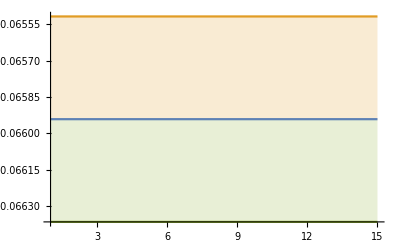

```mathematica
Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,15},Filling->{3->{1},2->{1}}]
```

```mathematica
SpoilHWFLOPlotN3=Show[Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,Length[meanErr2[[5]]]},Filling->{3->{1},2->{1}},PlotRange->{-.2,0}],ListPlot[{Table[{τSteps[[1,i]],meanErr2[[1,i]]},{i,1,Length[meanErr2[[1]]]}],Table[{τSteps[[2,i]],meanErr2[[2,i]]},{i,1,Length[meanErr2[[2]]]}],Table[{τSteps[[3,i]],meanErr2[[3,i]]},{i,1,Length[meanErr2[[3]]]}],Table[{τSteps[[4,i]],meanErr2[[4,i]]},{i,1,Length[meanErr2[[4]]]}],Table[{τSteps[[5,i]],meanErr2[[5,i]]},{i,1,Length[meanErr2[[5]]]}]},PlotRange->{-.1,-0.005},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]],markerlist[[4]],markerlist[[5]]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]},PlotStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau_{\\text{steps}}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3(\\text{mNLO})",Magnification->1.2]]
```

-Graphics-

#### QCD NNLO - gauss

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={393,393,393,393,393};
NWalkers=200;
Nf4α1LoopBig={0.225626,0.225626,0.225626,0.225626,0.225626};
aList={1,2,3,4,5};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
csvData=Table[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"],{xx,1,Length[aList]}]
```

({mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.10298068285388369, -0.10083440563228889, -0.10229007733381226, -0.10522269502911838, -0.10351719224192778, -0.10475652049265191, -0.1043430597562423, -0.10169963833201354, -0.10336600359887395, -0.10555934599053637, -0.10441763994527639, -0.10283317178092145, -0.10451300281859247, -0.10874195968144972, -0.10731861506184673, -0.10870708318580626, -0.1038302703359219, -0.10594447051180965, -0.10834486343448343, -0.1074962394674518, -0.1086605260897322, -0.1077920494868556, -0.10875941606585261, -0.11028032533609028, -0.11818348921158707, -0.10685067838976091, -0.10226045706393835, -0.10388371884802444, -0.10455833950886692, -0.1080539935367016, -0.10601251906038292, -0.10026191595048993, -0.10105529975174674, -0.10233460583026012, -0.09866470893125816, -0.0996679905600765, -0.10033770817252027, -0.09871882364765373, -0.10011909774324357, -0.10053143366504566, -0.09946982981888712, -0.10306810568973548, -0.10547695448994042, -0.10740634158820972, -0.1143964861588604, -0.11089625695544232, -0.1032222972574858, -0.10363186492495725, -0.10684064691274883, -0.10814174544999978, -0.10756384671207353, -0.1043146007336, -0.10713055048544771, -0.1133209248092941, -0.10693775072830444, -0.10971595671244298, -0.11082938081365534, -0.10761691814655104, -0.10461331126641434, -0.1050351496820317, -0.10448570536269314, -0.10482263185420165, -0.10608234685238173, -0.10781695920243536, -0.10917772370835561, -0.10481050077532861, -0.10786207987620974, -0.11133833267923313, -0.11039095616587885, -0.10575432217211256, -0.10801630459855671, -0.10748704234741464, -0.10609875480373063, -0.10502179146194605, -0.10289577322293439, -0.10386982855871042, -0.1036393785333988, -0.10009506004781542, -0.09951883804022953, -0.10254891287601739, -0.10352738921616966, -0.10490796948670907, -0.09977545964504513, -0.10098480320759566, -0.10089099119151142, -0.10195027786100191, -0.10984446643828538, -0.10179904341593989, -0.10329762219710051, -0.10221693500956912, -0.10321379268417105, -0.10140495801604342, -0.10152118502832805, -0.10328951730503447, -0.10220661137785561, -0.09914727055984389, -0.10099943352693734, -0.1024550507945211, -0.1039947996240408, -0.10240169474398882, -0.10314614398193575, -0.10239702906090653, -0.10329084139481508, -0.1017569053109795, -0.10310784287913378, -0.11046122363177152, -0.10415305140499133, -0.10417331139051171, -0.1108270570181519, -0.1041298177584143, -0.10833916099180171, -0.10637474465654917, -0.1073038485195185, -0.10682186249762053, -0.10420136062069234, -0.10481487184599024, -0.10698776344024072, -0.10174560334525923, -0.102789132084827, -0.10548129782800808, -0.10196000243494778, -0.10047745076331602, -0.10287126920858687, -0.10584877917422583, -0.1021176604935575, -0.10079241853204743, -0.09779322159796847, -0.09779304907222154, -0.10200534485708639, -0.0999780070529454, -0.10430190421236037, -0.10508945342533363, -0.10014059096020379, -0.10070351677456271, -0.10048864395350866, -0.10257036482222871, -0.102127428489602, -0.1065344140046576, -0.10380910402772736, -0.10632074715573014, -0.10264237291815297, -0.10681809250271154, -0.10715239680077095, -0.10859455797619345, -0.10782343048674937, -0.10493457948769397, -0.10472761469597919, -0.10467206136123967, -0.10630807770326235, -0.11066139577763247, -0.10745365005897463, -0.10153622876678157, -0.10502359366927554, -0.10471824124803013, -0.10206116884955031, -0.10437996241469398, -0.10399801705770773, -0.10772129120752866, -0.10923317991400093, -0.1175593001412301, -0.11783806296747264, -0.11443048100074367, -0.11102883169311073, -0.11116718087683745, -0.11622185093425413, -0.12884164919857338, -0.1232859477675748, -0.11726901700393472, -0.11370022576366474, -0.11485976274011332, -0.10901901318668267, -0.10728706607884342, -0.10595093661025946, -0.10526011862607655, -0.10987735683572807, -0.10830801962896525, -0.11295654995394508, -0.11076705465217754, -0.1145564030804409, -0.11939918287246962, -0.1235158363614788, -0.14922104524008636, -0.15772816485037058, -0.11834295157898546, -0.11465571834391958, -0.1086018435662303, -0.11332105963169745, -0.11555967669399961, -0.10993290586616476, -0.10378967167046561, -0.10172415018599336, -0.10836488549410803, -0.10354445721419608, -0.10709987959074256, -0.10030830221329129, -0.10023853905708663, -0.10426618939563366, -0.1050900632410584, -0.10171204052435798, -0.10291075540037194, -0.09590777133457826, -0.09402958890233208, -0.09346847474260941, -0.09562225556191133, -0.09420422359038802, -0.09403425054276827, -0.0948192338010562, -0.09620257122228001, -0.09531881020186769, -0.09704565190637453, -0.1032285818307777, -0.10052804372259563, -0.09864813425640144, -0.09746764185203266, -0.09572850040709427, -0.09746876229923274, -0.09973309047442448, -0.09723517490973822, -0.09765735070855343, -0.09934795088810981, -0.09943054876452506, -0.10187514230976398, -0.09878703669886976, -0.09572819901332616, -0.09723973159690977, -0.09554501356953486, -0.09701652883493853, -0.09766029547868244, -0.10226216089689444, -0.09961026246991513, -0.09946309367879055, -0.09586957816751941, -0.09586186327992312, -0.0973726518285398, -0.09456834093326809, -0.09560533380109704, -0.09229827830894052, -0.0955160481914298, -0.0960155003976671, -0.09548660077213049, -0.09216431205053767, -0.0919703318020868, -0.09368892464622532, -0.09762259666340377, -0.09714622954783564, -0.09671310677052854, -0.10239162459064463, -0.09868591792738134, -0.10365277587745159, -0.0995262141436673, -0.10040107040962126, -0.10500744913774736, -0.10409106220587548, -0.1030989537580254, -0.10056400056644262, -0.09812348997454444, -0.09680146030413513, -0.10308805764297412, -0.09926836620537888, -0.09801137561383064, -0.09779923190463266, -0.0971522427387225, -0.09990366518765662, -0.10260456207666815, -0.10259181700773697, -0.10581135625037696, -0.1148079705326222, -0.10540837668593513, -0.10103866522852993, -0.10270243037357128, -0.10087097943668634, -0.10352260884549686, -0.10019394677464896, -0.09972601721405241, -0.09956739294057138, -0.09979518031805122, -0.09849715137872618, -0.09780353604269443, -0.09912327375032975, -0.0993416298560369, -0.10001645707587387, -0.09861692091864123, -0.1002378141587618, -0.10170098518277555, -0.10272365107454659, -0.10333573799541382, -0.10308251693628294, -0.10170288895472411, -0.10182099447735038, -0.10739338503087185, -0.10472400353750422, -0.10573473507884282, -0.10578075990837683, -0.10443054850614858, -0.10939100715780065, -0.10956522271181846, -0.10883073863053677, -0.10803326831339198, -0.10435338367946467, -0.10172557961939524, -0.1046176215557688, -0.10956168003784152, -0.10675051124584914, -0.10215009805222175, -0.09971779125904104, -0.10375108838640658, -0.10776502820274234, -0.10642780156834726, -0.10894200162446362, -0.1085990395832782, -0.11490688342590173, -0.10862955758787084, -0.10974574120847044, -0.10824139597792685, -0.10862703762903224, -0.10425350180210749, -0.101808573145453, -0.10901767112040682, -0.10768190019675646, -0.1086562313437925, -0.10882140470849702, -0.10797333843491837, -0.10303905523129968, -0.10165808926771247, -0.10021403053970473, -0.10128681067808633, -0.10043083654503589, -0.1098408067364665, -0.1074850441242394, -0.10267192951574819, -0.10408053534606553, -0.10362060591227279, -0.1023080970462622, -0.09936345074878601, -0.09845619183472108, -0.10467233613389197, -0.10254357854986143, -0.10692628146920524, -0.10498306944992242, -0.10144252523064182, -0.10192809207906607, -0.10810900307333828, -0.1112576844636804, -0.11789290545096118, -0.12358394691978138, -0.12243289720731347, -0.1308989226820971, -0.1214938802046655, -0.11417858252130941, -0.11470966141523072, -0.11405105470136567, -0.11740235935431544, -0.11568597968226513, -0.10172582921441549],[0.004256052720424549, 0.0037490516962403156, 0.003796938445453477, 0.004553663371331132, 0.003766427718672288, 0.0045993820007573455, 0.0042724850300801575, 0.0037297073199786036, 0.003942041095796654, 0.005097510359937841, 0.004389843001428673, 0.004272571292944441, 0.004705513126501737, 0.005777343010809738, 0.006600966616970164, 0.007668965583781799, 0.004939261721159144, 0.0048381473254385885, 0.005392235313384025, 0.005125638530552322, 0.006017632637906608, 0.005080006201060901, 0.006302461971726793, 0.006561108449607903, 0.011629560248695794, 0.005203657553310556, 0.0036694877976126104, 0.004262272859737252, 0.004221296967335689, 0.007845631580068926, 0.006118609369002929, 0.0030555105705582044, 0.003589595563721654, 0.003646056216121475, 0.0025522086479142425, 0.0028463691035708035, 0.002925397302442528, 0.0028632130158018697, 0.003291423258070616, 0.0036979464541154927, 0.003053380437909483, 0.0038400980407440103, 0.004090097519846813, 0.005177021785443969, 0.010189215014944242, 0.007457612211668034, 0.004045934110953241, 0.00414214917567062, 0.005388913395944732, 0.007128043862024469, 0.006307092070563398, 0.0059713606998444135, 0.007151342719858385, 0.009957280776008047, 0.005499460277852501, 0.005516902805518074, 0.006093036978870088, 0.0052255869808828835, 0.0039465549565499535, 0.0036209389253829597, 0.003459549309520176, 0.0033522859822329156, 0.003555864521221542, 0.004163304407463216, 0.0043201137306369645, 0.003813816578830447, 0.004867545055278434, 0.005913397274224417, 0.005140919798286183, 0.004316891651286073, 0.005295718228980662, 0.006101078178746602, 0.005638632682318692, 0.004328935441552329, 0.0036616974756664964, 0.00383491208383121, 0.004924631483906635, 0.004664894483016601, 0.0036606769111968565, 0.005637445351255652, 0.005612775781713168, 0.006854141047130976, 0.004031446710928797, 0.0038796291632486163, 0.0039941430635422395, 0.004664218627630647, 0.008523685548041131, 0.005155139278172443, 0.006322032043082591, 0.005291705093006995, 0.005677340757737909, 0.0052251955678942795, 0.004628838063208786, 0.005587699418478629, 0.004454408195707958, 0.0036543443237041164, 0.0037326300404963548, 0.0039562537333629995, 0.005180902548660089, 0.004428349399615156, 0.004351844054674781, 0.00533159442454545, 0.00516129415402529, 0.003924097737400011, 0.004816153096776238, 0.010477425356546782, 0.00530023308938501, 0.004825966543738449, 0.011012559884919774, 0.004476680654372414, 0.0051054989169673545, 0.004794200449602405, 0.0047920696462980215, 0.004546036870178253, 0.004381314759454973, 0.004294267628962033, 0.004856012327181605, 0.003276881106377055, 0.0033522555723432537, 0.004383002039944439, 0.0035391725571487886, 0.0032651576889988466, 0.004157966882479084, 0.006907350113568348, 0.003431882606312597, 0.0037890585660428993, 0.0024943035180206917, 0.00261089015601912, 0.0034461692146342295, 0.002950413139777124, 0.004401530809448731, 0.004688337906721676, 0.0034795959521947833, 0.00353846626519554, 0.0035866575874244464, 0.003235066766971626, 0.00329147092501932, 0.00452296052713333, 0.003959891211574681, 0.005638507004756917, 0.0038072971275999734, 0.004790167225975775, 0.005121251715832562, 0.005640504450558593, 0.004941528276113275, 0.00447729322315216, 0.005186284276421613, 0.004559439343801123, 0.005579925416174841, 0.0079754958123172, 0.005293583125977903, 0.0038069825396979604, 0.004142524962626492, 0.003998948609566853, 0.0035110256498104434, 0.004211910628858766, 0.00427700252049627, 0.006285218847983417, 0.006988242716746188, 0.009562158993226277, 0.01070593000855323, 0.007699002103389047, 0.0070887489717984436, 0.006292581073813461, 0.007471584710292427, 0.015021751435226265, 0.015102638134767235, 0.01106061686566557, 0.01060876356752647, 0.010120160334910895, 0.0068306623314638715, 0.006897830445235275, 0.005697999073239185, 0.005572871214690925, 0.007078567624273322, 0.006726467783218329, 0.008770714735088146, 0.007780184252343361, 0.00923782994118337, 0.011572108093625206, 0.013187330993038085, 0.030936355965109342, 0.0408832575271064, 0.011179996102725173, 0.010069904880735489, 0.008079569960968506, 0.012351018024908027, 0.015127918995168958, 0.011124835144122791, 0.006134268697388151, 0.0051661205235260035, 0.007281034621272417, 0.005708236627768815, 0.008506033961075118, 0.005293991785409946, 0.004860069389383486, 0.006480624401678795, 0.005996031637921728, 0.004789476867959655, 0.008876678806978913, 0.0027555600587937947, 0.0027227893249372986, 0.002446911923091883, 0.002794881596568897, 0.0026997263856533152, 0.0031884469345030576, 0.0035054206678114025, 0.004085726226418102, 0.0036228838113248063, 0.00395307732973103, 0.004750082413474041, 0.004208267568817053, 0.0032530769668663068, 0.003006234622940126, 0.002523884220250595, 0.003067459120632095, 0.003602175357914832, 0.0027511149239090866, 0.003804348044942484, 0.004478976836358946, 0.004908303248646662, 0.004586985489100219, 0.003959656326418873, 0.0032691065207575767, 0.003374562448250477, 0.0032708729142356986, 0.003408906903622732, 0.003923417026423316, 0.005293694225065542, 0.004221749753805635, 0.004655125310855835, 0.0035098462653461726, 0.00378296540697736, 0.004601132686334805, 0.004257139476567022, 0.004769272663648183, 0.0035633344141702554, 0.004988526163775167, 0.0057912599582674, 0.005508304020383269, 0.00341992988547656, 0.003208772212172266, 0.0034610688376496925, 0.004344088601675549, 0.0037930636412295397, 0.0037068544654413863, 0.006596619072040427, 0.004419376870966154, 0.007961616168592799, 0.004696926005216892, 0.004475596973709917, 0.006962579256306699, 0.00644727999238268, 0.005909247993009031, 0.004624013600431008, 0.004525141799245205, 0.0037582845086476468, 0.006708743229765907, 0.004526425488679179, 0.004175655006044521, 0.004287543776248349, 0.0032509383096118874, 0.004757372358959332, 0.006195114797788064, 0.006982967257831012, 0.010913173196750638, 0.019857366793444145, 0.00971253998887701, 0.0054301800971403935, 0.005471828656775515, 0.004878205858228506, 0.006010365181329618, 0.004089707571445216, 0.00378399865076091, 0.003969823619356594, 0.004743597525182872, 0.0038527398997512084, 0.0035033124308035553, 0.0035890103904102836, 0.00404088515188635, 0.004280999035967804, 0.003602066349204494, 0.0036355088991735208, 0.004455366992306109, 0.004568855188083297, 0.004810960769769051, 0.004612306081727354, 0.004283265885565436, 0.0035421942829267474, 0.00432618769609471, 0.004302046759972283, 0.004619452430088184, 0.005317427277764361, 0.004522971299422772, 0.006546147048548608, 0.0075862185337055126, 0.008237141894657105, 0.00859856085524819, 0.006909323548230687, 0.006372163750263827, 0.007081552487529656, 0.012389277158381076, 0.010307180910338233, 0.005407493463530391, 0.00485674620214712, 0.00526375850518868, 0.0062156208696100305, 0.005592425651406807, 0.007841604798528608, 0.00796646119624856, 0.013112797525749967, 0.007790575195344984, 0.007971403178674319, 0.006921461764706374, 0.00799890105367751, 0.005375134548536745, 0.003771752923003006, 0.0051005268857922245, 0.006138558777138018, 0.005943861701819685, 0.006285225446714485, 0.005122883551910717, 0.00376046034344002, 0.0032760794535938768, 0.003254871198690387, 0.003977788300618147, 0.003659479835436771, 0.008587627115906268, 0.007409661444789563, 0.005500679801102058, 0.006224181362081167, 0.005440032592311586, 0.005784025280395076, 0.004591798261269065, 0.004289420684393029, 0.008108417584991015, 0.005613914717212699, 0.006895467998649038, 0.006671503070507629, 0.005318602824287803, 0.005163260057170749, 0.007335600348299317, 0.00873603708191849, 0.012732908573267481, 0.015413435373862415, 0.0137054811577856, 0.019447084312727823, 0.01000222778623294, 0.008051351616820423, 0.011762011224155875, 0.011992875297439101, 0.012676322906482358, 0.011481159074429415, 0.0036081746895689298],-0.0958243,0.000442399,0.888647}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.07454500042024226, -0.07440200868666054, -0.07519958553451621, -0.07631311901207616, -0.07634167611950643, -0.0760873934855968, -0.07581557942507491, -0.07656152568677833, -0.07778451528752145, -0.0768720085499282, -0.07692285147119805, -0.07641131602344976, -0.07514639855081906, -0.07507654244403729, -0.07527627473721037, -0.07587297690192923, -0.07631452616277937, -0.07613334561146806, -0.07640453697841353, -0.07586913099930523, -0.07662563174141213, -0.0764805931625104, -0.07631693146732904, -0.07597334391717374, -0.07658843227610604, -0.07857890237345556, -0.07673243871959211, -0.07813707709014643, -0.07822347999832607, -0.07812057348291965, -0.07803957401376774, -0.0785372654818177, -0.07981380337211348, -0.07918162329733518, -0.07877083525440713, -0.08041349368258334, -0.07942013412190192, -0.0787582547740576, -0.07728319801781552, -0.07662146029756352, -0.07612703444302037, -0.07780846447821534, -0.07965762346799675, -0.07982686891802145, -0.08044049915658533, -0.08122869371055147, -0.0808353674893592, -0.079996839449113, -0.0789490579201831, -0.07919563137166186, -0.08136803368429953, -0.0806772533234418, -0.07966197221442778, -0.07906180113450488, -0.08118273995609927, -0.08049067434209277, -0.08066792737855401, -0.081464320940136, -0.08186478035448042, -0.08236049270389724, -0.08096470012815891, -0.08032766965423475, -0.07914418183227467, -0.07871841974834642, -0.07855799550464035, -0.07778527265810332, -0.07821341128056811, -0.07872327418965275, -0.0794052872206472, -0.07864321578183699, -0.07776812410830194, -0.07757578033501812, -0.07842664947106483, -0.07835800048177112, -0.08007422049808303, -0.08204704641500667, -0.08128144910487119, -0.08123568107603346, -0.08367698546690788, -0.0886968191258565, -0.10680811856297569, -0.09192472577907246, -0.08743524278045878, -0.08556445962461749, -0.08602731872577281, -0.08638239551734692, -0.08384455172772592, -0.08169420978869728, -0.08101390818362154, -0.0809419756693669, -0.08178625825326487, -0.0835927246965147, -0.08344468580556168, -0.08336891749430902, -0.08680160684755846, -0.08578983880728516, -0.08823614138827827, -0.0876371713324958, -0.08985010875577801, -0.08996790887011302, -0.09107558604946821, -0.0893644432496749, -0.08920066619248058, -0.09117367177435826, -0.09135026691160593, -0.09154391618874383, -0.09397399682998121, -0.09491078016307476, -0.09339230634391002, -0.09047317955762799, -0.09107754852337746, -0.09012161226041941, -0.08818209042261556, -0.0882309503761076, -0.08741486090681459, -0.08986787308148954, -0.08952315470949532, -0.09020898753170863, -0.08921752075804885, -0.09064652343022919, -0.09158127479777901, -0.091554973563779, -0.09535264445322915, -0.10268200652178333, -0.09574910069161743, -0.09668529357746049, -0.09569763386994612, -0.10199164891408918, -0.10081592425899186, -0.0986611857440111, -0.09681024648443821, -0.10256528513288608, -0.09790575122674222, -0.09618709900561005, -0.11308355020157385, -0.1241007388135847, -0.10484361504052737, -0.09958704270531787, -0.09919215969567467, -0.10253118966067341, -0.10731881452982214, -0.11970186640636435, -0.10419003651514788, -0.1043289377974225, -0.1159359911470875, -0.10628992077717311, -0.10115571077131942, -0.11940591872992735, -0.10340924026540152, -0.10977244142108514, -0.10711326102833653, -0.1056591521224996, -0.10345218829482922, -0.10003834714557297, -0.09887957224208149, -0.0965992503894072, -0.10170032411481554, -0.0995818072790354, -0.10008975114385603, -0.10850460522248138, -0.10291232952559547, -0.10375348597935756, -0.09953810298178081, -0.10230115661028699, -0.0988101956860084, -0.09656908995282586, -0.09193265353485924, -0.09323393972201166, -0.09682806581410083, -0.10422901356455125, -0.10779909879328047, -0.10792703568858546, -0.11975210879968282, -0.11026956518198093, -0.10452549477903157, -0.10079559690303319, -0.11094326170063934, -0.10310351792625601, -0.10040513013206412, -0.10527306974737488, -0.10566377684483341, -0.1248571397047436, -0.11393850311969067, -0.11611168158275095, -0.11033238561697153, -0.10215763527734048, -0.10375967201546973, -0.10394985140046252, -0.101966381599904, -0.1009608223482329, -0.09694189556693189, -0.09225521558287374, -0.09147993118058964, -0.09256022748158388, -0.09139171163835803, -0.09025535936080643, -0.09107414241573814, -0.09064012451515376, -0.09098878724050512, -0.08971096729789349, -0.09284452940520793, -0.0942570145453718, -0.09526003291961327, -0.09850600818350576, -0.09859436110098904, -0.09763233875690515, -0.09467026376102297, -0.09637390520768085, -0.09980697744370107, -0.10127116649395497, -0.10125173299943777, -0.09989532053587596, -0.09727123808619789, -0.09463868063659507, -0.09086606308547475, -0.08901644594472666, -0.08777236880219774, -0.08727058632056232, -0.08698914395873664, -0.08777251677165206, -0.08411451977340408, -0.08702681105518063, -0.08552963925235121, -0.08320578157618022, -0.08370673364820254, -0.08169007126690767, -0.08066599506809663, -0.08018929538136456, -0.08244624416472188, -0.08162268543277815, -0.08230616439884005, -0.08269369974474441, -0.08316079720354332, -0.08260122746214187, -0.0812546805708107, -0.07990963776095704, -0.08138807036660785, -0.0832133769977136, -0.08495354301943096, -0.08441369170582264, -0.08535185283061453, -0.08426607971656899, -0.08436882434898474, -0.08697735101295834, -0.08735854838588215, -0.08755119360162304, -0.08859857884817303, -0.08813268219924109, -0.08775145718170871, -0.08534427678302439, -0.08490847957513621, -0.08217087544806927, -0.08306759665729811, -0.08225394873479072, -0.08108344970078842, -0.08033370329023012, -0.08089661367809148, -0.0816983869615566, -0.08206879578513071, -0.08282360608760106, -0.0849509710074015, -0.08548441113169797, -0.08564061485227002, -0.08579029399556015, -0.08573446888843608, -0.08423306402917877, -0.08403123987798401, -0.08577072667398473, -0.08489918653839515, -0.08322358208022385, -0.08449461554974458, -0.08425144647167124, -0.08385521775588106, -0.08594980840853, -0.08443637474114347, -0.08667932066864897, -0.0883084394812935, -0.0880932864290443, -0.09396129448593318, -0.09041547045255251, -0.08824398371729926, -0.09069675834446073, -0.0893485258367114, -0.08850034734012975, -0.08865657417919992, -0.0912154181766923, -0.08913390279347091, -0.08662696013950702, -0.08555035389338157, -0.08820285314880431, -0.0899233126892321, -0.08970348866040967, -0.09224419339526316, -0.09179217820249319, -0.09314950981432249, -0.09076876085530867, -0.09257709243254644, -0.09311177386153996, -0.09303476110251688, -0.09407075073993865, -0.09293246858936152, -0.09296473943680345, -0.09432290547749382, -0.09615592193077002, -0.09420384408752074, -0.09284771161178103, -0.09684549417895191, -0.09803498128922039, -0.09672315840458717, -0.0957089583476902, -0.10084388200238947, -0.09687905755537204, -0.09660839210338151, -0.10093066089734523, -0.09865649993442342, -0.09674264178676445, -0.09468667372959928, -0.09128067290059508, -0.09253879696426501, -0.09418443808061569, -0.09195092181486705, -0.09344623682562728, -0.09340355267028833, -0.09259019943032025, -0.09060942400636647, -0.09060313546198868, -0.09120987237418127, -0.09209148047092275, -0.09495893639770867, -0.09264484328045584, -0.09510678945802478, -0.09442518909706599, -0.09136313040358737, -0.09083105381333939, -0.08770803859675255, -0.08637105629634756, -0.08606813877763078, -0.08520467234079071, -0.08358466934187858, -0.08486785788313135, -0.08238317506212003, -0.08167988256292355, -0.08145354857342059, -0.08530508549764734, -0.08495437494729383, -0.08540968591463279, -0.08489680268557548, -0.08360274316095972, -0.08296878465939049, -0.08499908803133845, -0.08619420401454868, -0.08699528411922283, -0.08718934008393338, -0.0839457501199834],[0.0025248629806702834, 0.0024237624806425937, 0.0025329145486932786, 0.003064935770332996, 0.003322870151556906, 0.003243851709309135, 0.0030475053719691775, 0.0033335537949882644, 0.003638530832930723, 0.0032102268561287153, 0.003265205507906051, 0.002982051967041827, 0.0027229064965094865, 0.002616053793943764, 0.002662732033677347, 0.002927380751151194, 0.0031493272712417226, 0.002884234635406094, 0.0029065024705126033, 0.0029530288002031684, 0.0030656037765910992, 0.0028217830278638185, 0.0029458764303306544, 0.0028539509882418673, 0.0032392249302645266, 0.004107069799891245, 0.003352914546685081, 0.003909006238991071, 0.0038989204328992136, 0.0037622755515898843, 0.003970487731845878, 0.0041522756564407156, 0.004838829041546017, 0.004168225482704014, 0.004230103171658353, 0.005102644036187027, 0.0038655248700278488, 0.0035498914575678134, 0.0031784228947208254, 0.0028732394530142594, 0.0027421089545887987, 0.003186002053914002, 0.0037162537415965854, 0.003863629044560337, 0.0040785322421925795, 0.004276762006888401, 0.004159452489924072, 0.0037661834025497125, 0.0034380706985185044, 0.003771061413729027, 0.0042975143869083444, 0.004101358246278547, 0.003961282702275548, 0.0032895933181497695, 0.004207659775527579, 0.004132763993864105, 0.003736456917773088, 0.004038331729764124, 0.004133422621303482, 0.004680563382992196, 0.0043194551513015865, 0.004021926165969344, 0.003392954910603292, 0.0032082759572051424, 0.003119214467345148, 0.003086135636574237, 0.003193100193129567, 0.003201324817783079, 0.0033168220501739076, 0.0034260759093162297, 0.0030617371899918106, 0.0031044215507807617, 0.0031905200442226816, 0.0031748886948210673, 0.0038121689248536493, 0.004787746272795864, 0.004097626145672297, 0.004047965636040327, 0.005208277948529261, 0.007664271645451718, 0.02396597907837677, 0.009858100846369401, 0.0065932769018502676, 0.005445023400829779, 0.005770234864868106, 0.006291124071157888, 0.004701687215956391, 0.0037112370465552094, 0.0036080316310151523, 0.003555992505621523, 0.003606269767050833, 0.00419360055498346, 0.004138347326517585, 0.004221270029701935, 0.005841622093970027, 0.0049257413381940405, 0.006307753751814549, 0.006359899677463818, 0.007148382009936922, 0.006593825825750756, 0.007012975864686542, 0.005948526995531778, 0.00607550236406695, 0.006651627587182488, 0.007298798175798517, 0.007768804685129591, 0.009295898224103405, 0.009566023599616464, 0.008909025817737145, 0.006857824007500746, 0.006976639687247104, 0.00675332223029011, 0.005856725428232264, 0.006038031836034746, 0.005660044306747571, 0.007218359525991632, 0.006693669551616786, 0.00738713898506951, 0.006223443269512078, 0.006401563838567355, 0.006361843077103745, 0.006371819386900863, 0.007798702966676595, 0.013302799933004159, 0.008282491762012685, 0.009439815578500849, 0.009470160512090865, 0.014331528146519648, 0.012169729092460072, 0.01044966036950842, 0.009309948723578423, 0.014002306063201549, 0.010343185529819414, 0.010399077702324051, 0.02398674123187234, 0.03336785622938769, 0.015436055531254683, 0.010899817763960845, 0.011035934694610772, 0.012975069979425725, 0.01671038399079812, 0.026533200266800158, 0.01436882321899337, 0.015251605875044975, 0.02635281237798158, 0.018678481680030907, 0.012463601295846815, 0.025761525380730448, 0.014880982228471267, 0.020066811362384578, 0.017381237957936366, 0.017093897584806013, 0.01469874080675617, 0.011655999102857476, 0.010675059810062575, 0.009682984844547615, 0.01357435403790111, 0.010711848849547161, 0.009770691927736568, 0.015454043450996323, 0.01356076938967229, 0.013683959977993392, 0.011035551640719378, 0.01292099665354031, 0.009691420709421784, 0.008254226953814154, 0.006833659620246894, 0.007565792389130409, 0.010564289803680474, 0.014994917290322991, 0.017588603644827117, 0.017670852537860562, 0.027186204665222702, 0.020155844656660326, 0.01556883629305169, 0.013213887746924979, 0.020854020999092858, 0.014292036114372228, 0.011337622699792174, 0.013262571011229431, 0.013608635824300323, 0.02696490279518465, 0.018678025081453442, 0.020274117217995546, 0.015063823511211405, 0.010044725310228986, 0.01127042000754577, 0.01201692427394038, 0.012091010546882587, 0.010071304795321302, 0.007819324521444128, 0.005345550525289022, 0.0047742208302689465, 0.004614871589547583, 0.004557973494311783, 0.004992183097295804, 0.004393226856617542, 0.004513690575736761, 0.004836969207441097, 0.005470437243211185, 0.006061584825834133, 0.0063877724583256325, 0.0075557075673755, 0.009251105072693281, 0.010871638396606714, 0.01165252513859431, 0.00716955803430671, 0.00661427720221039, 0.007824893795223966, 0.007728546266273943, 0.008219155867266868, 0.0071019971167619435, 0.0063022948077682715, 0.0057511681797244914, 0.006085911073694436, 0.0058929462189125864, 0.00612009021184353, 0.006340053622889022, 0.006919109047313966, 0.007089130562603224, 0.005545545143672231, 0.007127804303918033, 0.00665844444524203, 0.005722828913347777, 0.005277085941157366, 0.0037886635654879497, 0.0031638856611879195, 0.002300990015291321, 0.002658304153707539, 0.0025904259747866866, 0.0030552767486208537, 0.003563870108163605, 0.005138249334762444, 0.00513875988333343, 0.004986208791386786, 0.005653787901603411, 0.004591386406992402, 0.004030843956301351, 0.004259801818108092, 0.0037879147802003564, 0.005340897987252048, 0.003761320001614956, 0.003520177394571423, 0.004781148112812168, 0.005593093744435149, 0.00588337824284323, 0.006425387901660516, 0.005826804910640484, 0.004491013544583089, 0.004128648766724727, 0.004518889131200649, 0.00402841561218053, 0.0032934548794141543, 0.00317917421608458, 0.0028046841182906247, 0.002742314212337154, 0.002750774692667401, 0.0032195767850820086, 0.003493799380642445, 0.004204602993891641, 0.0041577086570373555, 0.004152039928808455, 0.004869358540771118, 0.003775312015281828, 0.004109547422079085, 0.004518314819465899, 0.00499461310912039, 0.00553964569583748, 0.005337787685946198, 0.004445003744355925, 0.004191937276201399, 0.004131834059325445, 0.003752217078450104, 0.004188093270443956, 0.0041844581728389865, 0.004082079588561552, 0.004510882644221609, 0.004940478894820556, 0.006714942022799827, 0.006066473071044016, 0.00484749508852584, 0.005294471670453128, 0.004648508950699804, 0.004517097973105049, 0.00448587174989847, 0.005140803337839334, 0.004303651517078226, 0.0035993882194039436, 0.003680662105130783, 0.0045030705458808705, 0.004390433022807021, 0.004371138301857805, 0.004912308005282484, 0.00414454471186872, 0.004900552017567091, 0.004698264463275844, 0.005468677330925766, 0.005220695670926555, 0.005781064758490514, 0.006898166428386319, 0.006733615476766973, 0.008249130208012271, 0.007771007329439394, 0.0074975172427203165, 0.007187114066599976, 0.006579731676182587, 0.008483014326300975, 0.00833167421423591, 0.009627412766779852, 0.00907250922829396, 0.012197578206276769, 0.009077597955036383, 0.008961804050718643, 0.011610261435857019, 0.012177511950943158, 0.011342667319154589, 0.009046266973270047, 0.007940918208495223, 0.008586790814081069, 0.009173514147743521, 0.009244316309509469, 0.008988446989361383, 0.008298574409966937, 0.007770030554024742, 0.0073263242422508396, 0.0074157118408853225, 0.007232820653246986, 0.007489574473055665, 0.011253690320731837, 0.010961423157397975, 0.013968345471325357, 0.012932535590502054, 0.01181888506262577, 0.011383378311156314, 0.009393010797591264, 0.00826472486970301, 0.008650330697107208, 0.008178448055482877, 0.007761843016697831, 0.008061604662255861, 0.0064348208895951406, 0.006095411831665797, 0.0063358928038248835, 0.007427250807622143, 0.00788361834585846, 0.008052941829869882, 0.008300808408947495, 0.007269168983693417, 0.007169187723675976, 0.008136178383508875, 0.007809303829648915, 0.007910550782909734, 0.00737712940688642, 0.006771523809138924],-0.0751114,0.000866994,0.33495}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.05640741277715497, -0.05642757947789912, -0.056723529023363896, -0.05721801229461525, -0.0571825502907751, -0.056906309079538024, -0.057022174040705136, -0.05694077217240656, -0.05712071595942731, -0.05708627366519084, -0.05761199786885635, -0.05741557899580577, -0.05735706713997836, -0.057178480337631836, -0.05702773358036381, -0.0574213892754726, -0.057438577512675365, -0.057970241560448936, -0.05789266970231373, -0.05805278032155711, -0.058486872302424976, -0.05844645482973576, -0.058067230887245726, -0.05806502229509424, -0.057688501488829216, -0.05770837807761512, -0.0578912366115028, -0.05771176447083052, -0.057903723430411905, -0.05796671821210547, -0.05810954182720924, -0.05856583837283533, -0.0583450201414159, -0.05868264357343609, -0.05958106673798328, -0.059119999799174386, -0.05850326018022345, -0.05916166960647407, -0.05971014536497919, -0.06283922978143143, -0.06301273668551435, -0.06313395791656837, -0.06291488027604276, -0.06264513160293256, -0.06242431819427255, -0.06351427052971881, -0.06247530489613921, -0.06464701282232103, -0.06372728296753477, -0.063879972076427, -0.06592209405135177, -0.06436419592504788, -0.0628938605796381, -0.06723056114368758, -0.06565352146202752, -0.06806336814421154, -0.06639876424850788, -0.06499722634719579, -0.06693170393121163, -0.06911293505636523, -0.06780176503138251, -0.06742408611288546, -0.06725343801328178, -0.0665887933437215, -0.06719309977661872, -0.06630504361729798, -0.06452499317126295, -0.06403580611039711, -0.06398828739111552, -0.0639597550734742, -0.06355331091127023, -0.06389167898592421, -0.06297745216664265, -0.06281142204683005, -0.06346216231548153, -0.06335456155306052, -0.06367781158183895, -0.06359686232867649, -0.06328736726646637, -0.06341657745848377, -0.06335348995103637, -0.06347445262709253, -0.06393548165923578, -0.0632185491291865, -0.06290495019084827, -0.061974066830587225, -0.062017187003185315, -0.06249760667950727, -0.06239013613073924, -0.06164162599041016, -0.062354195357206724, -0.06220940870613561, -0.06163992654147384, -0.06265421569176927, -0.06280176611420692, -0.06337466484389996, -0.06304027688605149, -0.06294828346256534, -0.06276859982424804, -0.06275131311909474, -0.061889990981129364, -0.062176493604748535, -0.06217303105224855, -0.06205320645425854, -0.06211171346853975, -0.062098061098465676, -0.061640621488659196, -0.06172312187334087, -0.0621849006578438, -0.06225010457126986, -0.06237655131565514, -0.062279395165103404, -0.06168859667108807, -0.06190509799505808, -0.06234912654321733, -0.06342985453231934, -0.06404202363603945, -0.06439314260152598, -0.06397966016721868, -0.06404001615117516, -0.0650335080556378, -0.06640897447737468, -0.06738938552839212, -0.0688592889931005, -0.06657954531518204, -0.06795187780886054, -0.06840546548415505, -0.0692744003861149, -0.0685899864167809, -0.06849453981557992, -0.06889316678340389, -0.07114538709072124, -0.07110561298061632, -0.07122439769442138, -0.07574753381459973, -0.07428068270645995, -0.07333368096099094, -0.0768067075699848, -0.07804705281300095, -0.08002662343050743, -0.0815123341399502, -0.07755631447054477, -0.0743811091702316, -0.07196240622216696, -0.07344923494826952, -0.07222768211400923, -0.06955566077648943, -0.07222353417353332, -0.07098442722961991, -0.07205659692293098, -0.07237002134862315, -0.07422436322447203, -0.07582935299761448, -0.07354229648473579, -0.07336900931094273, -0.07408707975163964, -0.07532672625387879, -0.07418404447311376, -0.0740389029052483, -0.07678360088314909, -0.07848641826693174, -0.07829649398866642, -0.07696605737703677, -0.08017194954885279, -0.07913175723494394, -0.07836740326453516, -0.07594079234175437, -0.0755017771642241, -0.07808520992643625, -0.08536291083020316, -0.0856330735800641, -0.08342532778683752, -0.08598257237657493, -0.08094929319948595, -0.08300651633913642, -0.08087674449099977, -0.08419590753586298, -0.08155735286495668, -0.08229343833017248, -0.08421652857484443, -0.0830628404328737, -0.08622884152228631, -0.08441693936127466, -0.08765910686333914, -0.08547253766272461, -0.08160498955622132, -0.08328837230132523, -0.08250859994576061, -0.08232913073631011, -0.07958719032443537, -0.0792919607241555, -0.07850056854943252, -0.07693405259180291, -0.07653251418820735, -0.07528468480401054, -0.0752609111518441, -0.07649900965519807, -0.07584873494403291, -0.0754983702306719, -0.07479980086148007, -0.07533241309189755, -0.07530351313042058, -0.07386407725029893, -0.075010742967026, -0.07339082180157529, -0.07314906897168778, -0.0741049742091467, -0.07500917752685074, -0.0754009842346647, -0.07773207443037945, -0.07553532362190564, -0.07657914119573808, -0.07781858783007374, -0.07571623080069521, -0.0741907395646471, -0.07346687767671538, -0.07328355883389594, -0.07359344370673823, -0.07200661040057832, -0.07337276711850925, -0.07260956216319492, -0.07152357185859326, -0.07169913618740477, -0.07146414895584527, -0.07194439187292187, -0.0718889798969011, -0.07155638230770883, -0.07260237049544628, -0.07451139404139448, -0.07475103350819338, -0.07356333370812165, -0.07308020677775671, -0.0713254141381519, -0.0706936472154192, -0.06978328663142344, -0.0687447576652943, -0.07110081441404874, -0.07276156844619866, -0.07341649960082797, -0.07411612149380394, -0.07357191050850319, -0.07515776980003773, -0.07597104924951334, -0.07661218425870286, -0.0752732865141376, -0.0740620186584521, -0.07397182675181976, -0.07400507211123669, -0.07550311644573002, -0.07378277263998692, -0.07285860134765901, -0.07255497462930507, -0.0745263139353611, -0.07536314534727329, -0.07555438821551828, -0.07447892726426257, -0.07641757724278181, -0.07629726082152294, -0.07575290283807896, -0.07379042097202014, -0.07418247652296842, -0.07507961350989596, -0.07454977672615679, -0.07495865801101707, -0.07436305050209166, -0.07247944395392965, -0.07291812825439822, -0.07370068135984569, -0.0741581651949805, -0.07391578136663553, -0.07515848684336365, -0.0745280420582506, -0.075138932961392, -0.07727711488864572, -0.0777271365383097, -0.08022388894119797, -0.07895798875464974, -0.07742800368026201, -0.07968186405285099, -0.08055593503762734, -0.07971330094723657, -0.08316780310255698, -0.0816899148270521, -0.08217392478800543, -0.08172437473566779, -0.0836226231746941, -0.08155374279656045, -0.080030972410199, -0.07770804846131134, -0.07871929800345076, -0.07789832516542211, -0.07711225258724959, -0.07777569716799963, -0.07662925691315303, -0.07661301833392492, -0.07587609653090673, -0.07632553294263766, -0.07966744925142216, -0.07865747812428174, -0.07997461585121189, -0.08127662627277168, -0.07901273951631747, -0.07950710705784249, -0.07969153706776923, -0.07757090746988086, -0.07949711122452345, -0.0809875971038645, -0.08157030898492898, -0.07927032479243713, -0.07948602558600946, -0.0771921510137551, -0.08202663126950582, -0.08165799259131455, -0.08078139836011465, -0.07961338063017402, -0.07923993977516688, -0.07989186718406735, -0.07936590372759078, -0.08119036227794228, -0.0805506204815394, -0.07987071752647484, -0.08409264945164983, -0.08486350149209573, -0.0864373843616908, -0.08810641095445573, -0.08810359380241985, -0.09095766258160266, -0.09128624653956498, -0.1022460488767441, -0.10066171521102799, -0.1090009054124291, -0.11387672992463846, -0.11551753895473663, -0.12214482674869405, -0.10018271123277205, -0.09463751581189307, -0.10069801004897859, -0.0959403593786661, -0.09552099404377298, -0.09832730321030642, -0.09196242962630097, -0.09433578972178938, -0.09598315228181548, -0.10215044953615046, -0.1069937362213919, -0.11120640573071486, -0.11799728173869801, -0.10442736979778232, -0.1058033310296955, -0.11140056691836764, -0.1071366576155422, -0.107024076719967, -0.10706430032720034, -0.10756895741784886],[0.0016196141170265307, 0.0016616087775669867, 0.0017722975192096127, 0.0019753664841196004, 0.001901020097354866, 0.0018757294346873816, 0.0018773104234023872, 0.0018375325128517836, 0.001862194903769314, 0.0018039021707930297, 0.0018412126443219168, 0.0017604257078555233, 0.001776289008706909, 0.0017730744282419212, 0.001731381885034814, 0.0018377224710560767, 0.001881158301070858, 0.001952233279217562, 0.0018732950170587306, 0.0019203398898501836, 0.0019660155051496415, 0.0019128718603212203, 0.001861921831790915, 0.0019189384478132863, 0.001724506109254836, 0.0017337977973192018, 0.0018778137908989718, 0.0018016742823514546, 0.0018073932035170184, 0.0018267938065485577, 0.001977664747112352, 0.0020956429591175102, 0.002034087131233637, 0.002109979200553021, 0.0026251285460439262, 0.0023602925816746776, 0.0021784950749981556, 0.0026246428631998713, 0.0028802207177528513, 0.006042283474834277, 0.006020358880484159, 0.005804320531719391, 0.005314536599749327, 0.004570128038792874, 0.004563418628050515, 0.005440441970912985, 0.004502395202747176, 0.006365851198547734, 0.004849009118212771, 0.005024824938808576, 0.0061284250034612095, 0.005350892812738157, 0.004662143504919648, 0.00886220255782849, 0.007096683690080911, 0.009553091632135996, 0.008066053774784743, 0.006531466746933273, 0.008610557973608544, 0.01084416887606227, 0.009369635202719667, 0.008386933575858086, 0.007972918281246622, 0.007549855531984068, 0.007791213980547256, 0.007020605291699516, 0.005410151275584941, 0.004992670540892511, 0.004459194169978941, 0.004433103252002041, 0.004279301436047167, 0.004442182402244888, 0.003819709633789218, 0.003664237867829704, 0.003592465700527079, 0.0036521445139605065, 0.0036125789809916924, 0.003382812389374229, 0.003226358769930763, 0.003251017467978116, 0.0032839077211361846, 0.003303156283157121, 0.003415985189909475, 0.0031185736881129507, 0.0028225901548364746, 0.002582712328461599, 0.0025312047872859673, 0.0028462456749866892, 0.002803537806507853, 0.0024004839468576684, 0.0025351511754308363, 0.00255281929923641, 0.002372162065008128, 0.0030507532843757224, 0.0032071419878343986, 0.0033829369699123753, 0.003148398943367677, 0.002957712824964007, 0.0029053609409977355, 0.0029146233844649714, 0.002482538817508458, 0.0027211413308345644, 0.002602748510810034, 0.0025899320520823745, 0.002726601812102886, 0.0028648296888896868, 0.0025877223254892746, 0.0023375459688992238, 0.0023665018281777217, 0.0024043053777822415, 0.0023436041662539438, 0.002215756239973358, 0.0020139520093584024, 0.002049227312488201, 0.0023076905031734272, 0.0026164730839164448, 0.0028481204626028137, 0.0030747116909829227, 0.003165449202474031, 0.003104446865431627, 0.0035877890269798, 0.004336221536298682, 0.005317273025726101, 0.0065287541431880295, 0.00497972746021214, 0.005577932587557957, 0.005891918745430053, 0.0068249324444566006, 0.006519003168989652, 0.0059903576458370635, 0.005402338144786107, 0.007437575975311154, 0.0072279065797505775, 0.006738422525287276, 0.009845033289624492, 0.008526368504527147, 0.008191643596208359, 0.010681129924918997, 0.011695208787819843, 0.013045823699562179, 0.014958704291279606, 0.011422134000790351, 0.00917676807958426, 0.0073882229607972446, 0.008399037121718888, 0.00752233221660541, 0.005793638308025379, 0.0077053330217820935, 0.006426188069193594, 0.007181778332086902, 0.006911069416625717, 0.007916775220860638, 0.008674514053813483, 0.007375824560357488, 0.006834028946913269, 0.007261895043405814, 0.00801734059022458, 0.0069876306837294965, 0.007175051879176191, 0.009226843762977088, 0.010160812002575847, 0.009664255703420608, 0.00879030384834632, 0.00984259338119522, 0.008961574390911406, 0.008775871868849906, 0.007507446006224341, 0.0071885240068000145, 0.008430292735896879, 0.01219624240995952, 0.012778762117875764, 0.011019123646926676, 0.012866524863167738, 0.009958136049714439, 0.010830372733536374, 0.009488774261455432, 0.012167920202670067, 0.010021720594603765, 0.00960842533057651, 0.01044817636785116, 0.009639775528547796, 0.011132196810578787, 0.010441839006035404, 0.011471847432061007, 0.009229662850778595, 0.0075537205154184855, 0.008496462613789736, 0.007874550805144816, 0.00799905321673315, 0.007075816583607976, 0.006708647257996931, 0.006597716712859344, 0.0062676901067427225, 0.005682629877484089, 0.005136488746640814, 0.005864279078805804, 0.005826176342503863, 0.005088222771959737, 0.00474117493149559, 0.004687437814014864, 0.004512374586123602, 0.004532960179219114, 0.003850951318380376, 0.003936566132747918, 0.003675701282119997, 0.0035098729412738816, 0.003947630061688533, 0.004445504965860711, 0.004536593666050084, 0.005584854431325994, 0.004703470731284102, 0.00499080065250307, 0.006006131517061332, 0.004842900317277735, 0.004287162498903708, 0.0042611905748854255, 0.004161799695645978, 0.004642660992471249, 0.003703758308285473, 0.004181733009451429, 0.0039826401688625186, 0.0034188487764965953, 0.0036239593443902307, 0.0037627896911498816, 0.003544443967651936, 0.003295861594534408, 0.003085421600232426, 0.0035799875166980157, 0.004756534048236902, 0.004795756949780717, 0.004433121949212232, 0.0036954170275427297, 0.0031454333550120944, 0.0029259894970049315, 0.002935051999594147, 0.002489695997863785, 0.003367359424849529, 0.003949789757000265, 0.004094730213973645, 0.004017137389384125, 0.003911528731876338, 0.0048167854518570115, 0.00540291750380547, 0.005198096587290865, 0.0046950226413759195, 0.003837974748328412, 0.003739225088616002, 0.003733515629801692, 0.004368879886658646, 0.004124597085833978, 0.003802687399391683, 0.0034356699151873583, 0.004164628900232911, 0.004379523329291432, 0.004510256888050094, 0.004284905689245534, 0.004838145312320538, 0.004619040673523711, 0.004121194937415153, 0.0034216663872693996, 0.003689714169149624, 0.0039725976997476405, 0.003619526782243953, 0.0038759095213311266, 0.0036435443376319804, 0.0030862746980183735, 0.0032578353707057124, 0.0033586609851586776, 0.003342632650988373, 0.0032613910455417433, 0.0035108025443703473, 0.0031172685770091244, 0.003746618550989669, 0.005122635946968009, 0.0061253370890644405, 0.007185587634966578, 0.005354131523527812, 0.0044718465031282845, 0.00442759205565618, 0.005408937653556283, 0.005379236760602197, 0.00827077457480354, 0.0068039760769013635, 0.007941821768059056, 0.007091783187824896, 0.008128700584306193, 0.006840621488137864, 0.0062534318411452666, 0.0049184383642443975, 0.005327196376645096, 0.004947010424330284, 0.004455240489453301, 0.004240398278422701, 0.004462775855730135, 0.004936945016914238, 0.005262490534124182, 0.005750403399205998, 0.007843397885795045, 0.007428757976341526, 0.009008989456914172, 0.01048419461416715, 0.009045563703570986, 0.008664862276016027, 0.00876679484139785, 0.007897385432363407, 0.009040728001519343, 0.010246206881716334, 0.010267055337864234, 0.008918878263625038, 0.008962886994978112, 0.006713825799531921, 0.00965440090453061, 0.008854747681898163, 0.007196508331377392, 0.0064455762979205265, 0.00616245718698055, 0.005850468663753679, 0.0061682956260273245, 0.006758552040095102, 0.0072576886785422805, 0.008061130048918817, 0.010591169867546558, 0.011445046871852283, 0.011656667908111613, 0.012770016886786001, 0.012527843434052771, 0.013336607773903143, 0.012939378024656625, 0.02294981626418194, 0.021807514242106196, 0.02718697469066592, 0.03304470228797642, 0.035360931750753534, 0.041591705181673495, 0.022935177219186094, 0.017920256828948787, 0.02334522082742476, 0.018947101849785517, 0.017837220879430852, 0.01904546749872118, 0.015204271297964417, 0.016781598151155753, 0.01775192733661709, 0.02116571027302413, 0.025435952244122165, 0.027243349933885472, 0.0332977316450668, 0.023240816563352515, 0.02319510690970607, 0.028426598023640712, 0.024106974456616508, 0.02389311063825665, 0.02237195048951833, 0.02430024635691093],-0.0578416,0.000850435,0.370265}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.04724857268548678, -0.04731952059950838, -0.047824778775204246, -0.048437892037090306, -0.0487294559552423, -0.04873198988464832, -0.048363953946745954, -0.04837467287108159, -0.04868939163721037, -0.04850134465156586, -0.04847263384277376, -0.04855575839534324, -0.04832565329119422, -0.048466563094422044, -0.04835254061766969, -0.048465290613338166, -0.04839818643174577, -0.0488736391692594, -0.04867346250985031, -0.048390558483196434, -0.048804688520815716, -0.04888350748759371, -0.04851237369956661, -0.048339960894479686, -0.04829418034970166, -0.04823031335282761, -0.048146640260044574, -0.04863904243626609, -0.048772750671320184, -0.048817234482111664, -0.048583645159926504, -0.048575515473218485, -0.04856108958171463, -0.04896873704968809, -0.04914595319725315, -0.0490461601859121, -0.04915736016955858, -0.04945872720100883, -0.049353314814013755, -0.049517196476302226, -0.049361770217566284, -0.049842124707691345, -0.04968830190735783, -0.050367001728520794, -0.05039927557646555, -0.050760105113907356, -0.050721266493838624, -0.05094047067746083, -0.051191176520486555, -0.051190756926195576, -0.051874048871466745, -0.05154972858813811, -0.05094298390677855, -0.05109432824737507, -0.0509228632980361, -0.05040842841256958, -0.05077290265555649, -0.050510979287653794, -0.05021913041590472, -0.05017974794409565, -0.050425852104158043, -0.050796159245963125, -0.051179037675448624, -0.050889876060618025, -0.050802587191002335, -0.050609831226916764, -0.050825709991719814, -0.05154996529076567, -0.05143587130317596, -0.05103265788053356, -0.05107160258246431, -0.05106668146892963, -0.05121083977297087, -0.05138881312073833, -0.05166551958694657, -0.051093619622291274, -0.05109221679807842, -0.05110333950456966, -0.051604203134912034, -0.05157532764975726, -0.05191509239377429, -0.05226148436802761, -0.05246961003194246, -0.052281378987698406, -0.05215991260035943, -0.05191852499457943, -0.051830698375973934, -0.05173513041438565, -0.051493722186269165, -0.05147137217530957, -0.05176102837649946, -0.05179273700910676, -0.05123822897724089, -0.05178362204286569, -0.052611001237164244, -0.05285623377615513, -0.0523898499969341, -0.05287980549718181, -0.05316491307319987, -0.05347600210973474, -0.05338676173088204, -0.05379177868560854, -0.053287930035181806, -0.05303446868253455, -0.0530845617786334, -0.05337794593670697, -0.05317505422555589, -0.05337818735471054, -0.05344907421623458, -0.05352545006454015, -0.05376717615171676, -0.054294473989360006, -0.054531390444122474, -0.055137960267512984, -0.05642960750286326, -0.05778664433310162, -0.05774923476795923, -0.05936727696664961, -0.06000837489219463, -0.06003122610573565, -0.06173802025887402, -0.06392882529414311, -0.06569136938698038, -0.06965249435554252, -0.06731328481410644, -0.07011571769692089, -0.07217681856006776, -0.07476194148372349, -0.07132793945490062, -0.07263838987063817, -0.07311680869730042, -0.08110310095963885, -0.07229220068143138, -0.07361627358796193, -0.0829541597741706, -0.10043137348153634, -0.09956126507476945, -0.08124095509007405, -0.0852635215937415, -0.08389998883365127, -0.09506925734459612, -0.13671171522287257, -0.09779036805939546, -0.0900972920468718, -0.10455727300310165, -0.10203848143806817, -0.08763465603455603, -0.10549105366434405, -0.0876023706364629, -0.08947844337464787, -0.08727552205721614, -0.08686933859878015, -0.08534028674202204, -0.08146930578607402, -0.08022197843178948, -0.0797644390660155, -0.08493025582478436, -0.08038054048258031, -0.08133406705149031, -0.09245732458838384, -0.09210591331740792, -0.09231507056220788, -0.08595785508423713, -0.0877782083406927, -0.08214797422796365, -0.08192242127881344, -0.07967335395688464, -0.08212465772849463, -0.08776369643557844, -0.09656335610687701, -0.09939495572686469, -0.097732457859234, -0.10891269516478383, -0.09879075075852985, -0.0939585588044376, -0.09216370477482494, -0.10367169393087933, -0.09707854102865308, -0.09345280929311639, -0.09547376685596566, -0.09806422650353996, -0.11462058504176535, -0.10814988155639295, -0.10796966221437329, -0.09890944796999546, -0.09221981998735923, -0.09327858211899594, -0.09342572253628365, -0.09341829120679307, -0.09452631771431676, -0.08892354210680017, -0.08508710323188048, -0.08102128229922807, -0.08323885639955393, -0.08411525025647701, -0.08150188801180872, -0.08777746065216506, -0.09090887559028658, -0.08831711211448796, -0.08391302672903383, -0.08665999703471136, -0.08927158018351479, -0.08775031887011735, -0.08575608191216404, -0.08494126271444451, -0.0818512476576067, -0.08219215140506003, -0.08447808221218552, -0.08544097676252883, -0.08841392682267628, -0.08651697734008316, -0.09088044496804706, -0.09196055308059557, -0.08902222778993195, -0.08700594588760706, -0.08765321449315597, -0.08959528812497228, -0.09423112439921859, -0.08996731333706987, -0.09429199604799877, -0.08767081889930697, -0.08709337502986102, -0.08692311222421999, -0.08353105252854522, -0.08522584972197426, -0.08566487301679294, -0.08752740599492734, -0.08523782719839396, -0.08880384274930679, -0.08575471215283208, -0.08852079417263836, -0.08476452839935042, -0.08222803414337078, -0.08391738840533808, -0.08210654800362337, -0.08771233298586154, -0.09057866659166815, -0.09305992232134665, -0.09100005629040701, -0.0906156389410993, -0.09400668008238802, -0.08704984837391033, -0.08762509048182396, -0.08843143777563488, -0.085973685712671, -0.08554578669273455, -0.0840018337575541, -0.08644532190424327, -0.08890521930815591, -0.08426132266656942, -0.08148088918919233, -0.07841206573030461, -0.08018773953825087, -0.08139992836241014, -0.0816729776603493, -0.08151921331197251, -0.08311100265094656, -0.08196318340178319, -0.08050032317798492, -0.08109737392787596, -0.08334010929671623, -0.08740290648932399, -0.08384009069120124, -0.09054249204734702, -0.09105707804447777, -0.08977858582145315, -0.09260737465514393, -0.0991656411515365, -0.09904762972169115, -0.09520264658125811, -0.09569670512030731, -0.09365876911921509, -0.09230906553214267, -0.09341369311131845, -0.09393165325955957, -0.09818731348766539, -0.09618487260928353, -0.0977239910484746, -0.10079388544196698, -0.0998795043159275, -0.09699294945804364, -0.09621395776501536, -0.09303389511175576, -0.08868171623257227, -0.08618182580401561, -0.08835678458775506, -0.08888771561519496, -0.08640261385632488, -0.08400628566731566, -0.08526803284767678, -0.08739864495361009, -0.08528278121324347, -0.08914535395077271, -0.08920612650688194, -0.0913521193208034, -0.09155292282764163, -0.09127276413586799, -0.09067742261452821, -0.09076129765556681, -0.09047214366524911, -0.09075907505257322, -0.08925950367665658, -0.0919068833456633, -0.09591333707381759, -0.09632015436511197, -0.10565481191564086, -0.1146414346581881, -0.10774469362946161, -0.0995308043721035, -0.0942181134839411, -0.08964135689017444, -0.08873815418449542, -0.09065944410256967, -0.09179793022854751, -0.0863471497300804, -0.08625892125541351, -0.08797249527098458, -0.08400185774950367, -0.08170008843784755, -0.08033467464410245, -0.07951609260232932, -0.08044229215523387, -0.0820116073109926, -0.0807770858922739, -0.08246258900125455, -0.0818006966325285, -0.08558283591921488, -0.08691083371057932, -0.08454390184158361, -0.08456157966435807, -0.08169185817900637, -0.0828701051354002, -0.08143255997131753, -0.08219314779129275, -0.08082757362458559, -0.08013882533295018, -0.07796732593772317, -0.07766678602865322, -0.07840863772679887, -0.0795720519235739, -0.0823348961195725, -0.08329669256631646, -0.08329703643920534, -0.08263231116829532, -0.0785108701547751, -0.07912502542784154, -0.07769917604133295, -0.0747382921504551, -0.07378654969919256, -0.07196820037360108, -0.0727819637474005, -0.07319553317901359, -0.074370577146809, -0.07235773828395045],[0.001715052469957464, 0.0017807916634636327, 0.001983777420589589, 0.00226336743125567, 0.002262402647282181, 0.00230551348341531, 0.002207366441125252, 0.002229506271409793, 0.0023223788849020504, 0.0021994583873288422, 0.0021207959615860738, 0.002074880681920651, 0.001961629319875454, 0.0020299153083850954, 0.0019564258284621833, 0.0020402920717459676, 0.002055681308760727, 0.002194933581156245, 0.002035479414321216, 0.0018543949065382285, 0.0020014569146424516, 0.001981458196272927, 0.001894350115920666, 0.001825492306272786, 0.0017285796822922653, 0.0017287104695546754, 0.001685082616319835, 0.001864251680793189, 0.0019482276149897202, 0.0019380115046270852, 0.0018487913101187612, 0.0018660430678762577, 0.001839543782319917, 0.001971679961535757, 0.002075668344389615, 0.001978460889674923, 0.0019925984117458296, 0.002189623904066037, 0.002043058044722477, 0.002024402333656985, 0.0020071893978959865, 0.0021279300161105045, 0.002125282286655632, 0.002322393359467781, 0.0022561520279227175, 0.002375063209574647, 0.002357434047965978, 0.0024264097635711013, 0.002473729351234955, 0.0025060557725895944, 0.002952687863491849, 0.0026544577155578207, 0.0023406262582236666, 0.002434887215495181, 0.0023961545504298295, 0.002188136511893118, 0.0022054544843709044, 0.002028710880796598, 0.0019053168549434821, 0.0019110348773649425, 0.0019941431044569443, 0.002118423411995269, 0.002259939522740825, 0.00218317793713398, 0.0021051662266446318, 0.002073935134175235, 0.002124154836075867, 0.002361774963195378, 0.0022639975349553875, 0.002143458449680532, 0.002228617439626004, 0.002322959784545684, 0.0024056655177240025, 0.0023577281278613638, 0.0024193877110227236, 0.0021949362859411906, 0.0022147851565293814, 0.0022414339404806744, 0.002415986532431477, 0.002360283312594744, 0.002487221971652232, 0.0025292758378237944, 0.0025107393716213085, 0.002413085640328045, 0.0023658143618982023, 0.0022673947617820375, 0.0021982964622897167, 0.002146558793354638, 0.0021009823147429083, 0.002157254150655498, 0.002227986456543233, 0.002343477463855319, 0.0021157441947878947, 0.0022959287148197325, 0.0026142597178703676, 0.002801240736506423, 0.002619272406360348, 0.0027926893544557656, 0.003003161234050015, 0.0031585360415335054, 0.0032426450835228507, 0.003452790464785967, 0.0031404398305199927, 0.003036161568061393, 0.003084204960386053, 0.0032351362200901367, 0.003237993952358723, 0.003068114526232513, 0.0030579550607733063, 0.0030364576813563444, 0.003093714228683726, 0.003253460561988406, 0.0035508941528910286, 0.003844362987353125, 0.004680328112727533, 0.005124137298395586, 0.005121864406454803, 0.00598564495146323, 0.006366402173696255, 0.006257694784427508, 0.007502251034446579, 0.008689372950053079, 0.00978010875681802, 0.012928399202950797, 0.010916762354369846, 0.013477080408670326, 0.015352885663550045, 0.017195449434718815, 0.013334985281536435, 0.014513400989178612, 0.01404752923385128, 0.019645272578118923, 0.012717169391600463, 0.013621751017474355, 0.02076884308370732, 0.03566477238783557, 0.03424381973855232, 0.019274838896757962, 0.022012842006998615, 0.02130861336867204, 0.029062957380630708, 0.06013009266267666, 0.02829395577578383, 0.02239229612998652, 0.03462263809868823, 0.0298014726117788, 0.01999623146705115, 0.03205358097081575, 0.019221878257619052, 0.02245156543354125, 0.02099447207710937, 0.021023832290471944, 0.019852076503402375, 0.017073279355075632, 0.016069699132863876, 0.015460658031006193, 0.01879376471227146, 0.01613856989550241, 0.016528116537222252, 0.022812111885167914, 0.021217699318525084, 0.022034693463558745, 0.01833093196383396, 0.01955979994770126, 0.01616199781228442, 0.014997926615129529, 0.013483591957737455, 0.014310971308637432, 0.017059379685816105, 0.021868963165531476, 0.02400046402553833, 0.023527120828483516, 0.030700597177662894, 0.024603050541235936, 0.02177484844929629, 0.01935341003379676, 0.025355328966819815, 0.020266149680672377, 0.018058049148437363, 0.020100677930408727, 0.020701786273522316, 0.02964231809776663, 0.026909504609770058, 0.02628015799562684, 0.02187225817626495, 0.01704241825646677, 0.017952439903461053, 0.018061036860945446, 0.017922342568819367, 0.01615072991498091, 0.014022326079884037, 0.01147437539488015, 0.009782304720701105, 0.010298271360239383, 0.010823237722838469, 0.010455364755344703, 0.013213144886629379, 0.014661391692407235, 0.012906179444616205, 0.01101916676435836, 0.010925073953267254, 0.012184109779068218, 0.012602846934249156, 0.010907993815309436, 0.0104621141852057, 0.009430001610423951, 0.009232870029169475, 0.010072826851700037, 0.010414812448282585, 0.011884058577735675, 0.010985943693517375, 0.012644735440658892, 0.012486242272299755, 0.011398840234605398, 0.011744675144664903, 0.012456256318796355, 0.014341120247439127, 0.017244213467859308, 0.015397202332497924, 0.01755559186351724, 0.014588063500397416, 0.014270249744588325, 0.014596808874844687, 0.0118365995732149, 0.012675111212631545, 0.012577652613250655, 0.014093224302177867, 0.011776840411070048, 0.012709638046849103, 0.01150666184948382, 0.012741228355445701, 0.011306218352320133, 0.010264491137852898, 0.012688524927659239, 0.012663340953435716, 0.021045299595478625, 0.01992333560497362, 0.02009639183195159, 0.016203874749892593, 0.014898029692702689, 0.02006526571658751, 0.01167566378815351, 0.01121902814204432, 0.012509659953910257, 0.011563545022340803, 0.01076764081276712, 0.009444145629793736, 0.009389406390793328, 0.010162697371222993, 0.008850678048359352, 0.008334983308832214, 0.0077804767675503945, 0.00757460411846418, 0.007691833805384231, 0.007393107941730882, 0.007329398420198068, 0.00764874209174783, 0.0076642699524523475, 0.007457964462808526, 0.007033420755291048, 0.007369724550603153, 0.008297413996090637, 0.007302341546549126, 0.00912697764850661, 0.009604087166049534, 0.010926025193147478, 0.013221029151742478, 0.01912934193611938, 0.020740890243369565, 0.01812144823262654, 0.015296098556525625, 0.014061103564219265, 0.013548680869755423, 0.013034458301521487, 0.015394953097997063, 0.015194352473137041, 0.01249433971607598, 0.012670743992053956, 0.012340540222545422, 0.013059167900655805, 0.012841455595192808, 0.012382165055829848, 0.01014313743385475, 0.008871789459151083, 0.007757219739970803, 0.008091840387683574, 0.009277857254825406, 0.008274619859165954, 0.0075901159069374615, 0.0077436811670216505, 0.008507196036192252, 0.008081279305817956, 0.009013222679370965, 0.009448364386761379, 0.010278797149570728, 0.01219611564393022, 0.012652402075069211, 0.011844966935566716, 0.012817696954438738, 0.012390944095785283, 0.015062034150960335, 0.014710541908029062, 0.015430014551112713, 0.019935747602157907, 0.022618871815190237, 0.03135866350456851, 0.04018881965168066, 0.03164958345939782, 0.025646904473053612, 0.0217943396605383, 0.016741648671649047, 0.014064907368060703, 0.01584146558468235, 0.016753792714882563, 0.012194627164577821, 0.012337210143422334, 0.01292396312373722, 0.010748388053963541, 0.008211092144287875, 0.007989872306856865, 0.009762066348571345, 0.010013677573065467, 0.011442850564113701, 0.00809967190869461, 0.009677723293733, 0.008856784697747878, 0.010372044649349186, 0.010613814922151287, 0.011039535778729865, 0.01192522456750679, 0.011231034973989517, 0.01255462847465232, 0.011441727658250767, 0.01187372710037681, 0.009764190444466202, 0.00925608553164222, 0.008882600870884251, 0.00993336186052188, 0.011824995142979822, 0.012039312785841272, 0.014525924247558318, 0.013957268458733402, 0.014184446300113394, 0.01241853986657609, 0.00978280941652107, 0.010883854318037324, 0.010214665358065998, 0.008913758197184502, 0.008047172665964875, 0.007144960565552106, 0.0072259398925942206, 0.006498075313254753, 0.006433037556432471, 0.005652594064890743],-0.0461801,0.000857254,0.341812}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.040299434189476666, -0.040368870742184725, -0.040446848989275176, -0.040546988179359755, -0.040816513188323314, -0.04084043814870448, -0.04088250869010289, -0.040898916110454646, -0.04115997417487217, -0.04122659261387297, -0.04122514113020207, -0.04101744976133487, -0.04123056632357292, -0.0415039770410879, -0.04154206408449832, -0.041699793357878594, -0.04179648476457851, -0.04176277996870163, -0.04205991393166181, -0.04263355068550677, -0.042407694154886086, -0.04289327615710733, -0.0437162610436269, -0.0440508592421957, -0.04327841620852147, -0.04296413824803797, -0.04264186136089243, -0.04266112501826676, -0.042839355420848546, -0.04314346392217629, -0.0435298349178069, -0.04370325423040583, -0.04345523660546242, -0.0434696953784151, -0.04302142320012416, -0.042925712332038346, -0.042981380850952065, -0.042860939536958395, -0.04295807265329718, -0.043159842570218925, -0.04311152928449252, -0.04296188881675088, -0.04280900831347023, -0.04276678007765175, -0.04304589661024111, -0.04286245469609515, -0.043044283263266404, -0.043111849741847855, -0.04372330263679547, -0.04355380939569868, -0.043400138667178415, -0.043158278336300204, -0.04323374764261528, -0.04318178204653023, -0.0429005323272168, -0.04264094894521188, -0.04275252731960395, -0.0425345684436416, -0.042877541982875536, -0.042764593073896684, -0.04276369308065653, -0.04264735445772664, -0.04293258849848404, -0.04291216948293704, -0.043109706808465605, -0.042864364377074735, -0.04267568290142309, -0.042671738729830294, -0.043279620680561945, -0.04342753589161419, -0.04397727129540698, -0.044959557475314056, -0.04492244848515526, -0.044783395729634315, -0.04506994453865879, -0.045364677709068144, -0.045060582809181876, -0.045367679978664345, -0.04489034019839912, -0.0451847809303195, -0.045995703600611386, -0.046366380032504616, -0.04596655983787897, -0.04602403495073607, -0.04740302873072505, -0.047009728611656504, -0.04658450536267319, -0.04674569583281376, -0.047402872397463734, -0.04691233628767892, -0.04641679008792596, -0.046463944708717175, -0.04633958818508667, -0.04584802440368823, -0.04605735025795752, -0.046513119073738264, -0.046566403299858596, -0.04610147706672916, -0.04601489908659384, -0.04634313468719641, -0.04591806313760495, -0.045911737108536924, -0.04613576729277558, -0.04610281590715151, -0.04599857964109787, -0.04587028369244901, -0.046179407992643785, -0.04626320064636825, -0.04648875062518862, -0.04662677213082874, -0.04721417140959395, -0.047193784830444875, -0.047237169960788396, -0.046999047734542, -0.04701759107202717, -0.046657684571857906, -0.047106321696500864, -0.046783059504795686, -0.047432877247229145, -0.047776540117087624, -0.04782728332169303, -0.04773440000359309, -0.04752845645624327, -0.04724696982100465, -0.047466753983767325, -0.04742813603231305, -0.04663152759848448, -0.04667352892209099, -0.047171531487766004, -0.04730191831654659, -0.04749510626840142, -0.04725013606252556, -0.04768734131338447, -0.047755934605151276, -0.04775225978328554, -0.04803440401877728, -0.048216409702925636, -0.04738879080236187, -0.047585171002607916, -0.04779387872998354, -0.04779533779578197, -0.04789603469096644, -0.04763859476763689, -0.0484213168008362, -0.04852577713787815, -0.048740901152051805, -0.04944068128055067, -0.04969501265240094, -0.050912411773340084, -0.05039111877212177, -0.050757025613288057, -0.0496414864553882, -0.049562503158892934, -0.049535712340514744, -0.04982854054231373, -0.049104895412376816, -0.04945329757307318, -0.049632268851785885, -0.048781324021711245, -0.04932006724417583, -0.049092360548519204, -0.04916002069999056, -0.04912991862346311, -0.04927325840621, -0.04937436007016705, -0.04921698095867253, -0.04909043599143385, -0.04958823604475471, -0.050033020296652256, -0.05042518889010402, -0.05092742826748976, -0.0519094068346835, -0.05217924644693226, -0.05328295197779373, -0.05225537910428014, -0.05282887970233277, -0.05285233718210049, -0.05296420843793773, -0.052640806710403644, -0.05314721604183624, -0.054449542397999345, -0.05527877371900906, -0.05574437792524524, -0.05533538498673372, -0.05777267832466552, -0.0592593762110412, -0.05898028065994868, -0.058709232303400374, -0.05847943823038582, -0.05895239072783534, -0.06002096515653873, -0.05845661198782459, -0.058903824539871676, -0.060723376501148674, -0.061976332227024984, -0.06057694373722416, -0.059198269398766344, -0.05884597604303094, -0.059673110088244906, -0.057381597429974236, -0.061065724727726756, -0.06437569758117387, -0.06337299655185702, -0.06775220796853665, -0.065639265879504, -0.06383241283770465, -0.06294370796896166, -0.06323673299695269, -0.06384761913890534, -0.062391389352080766, -0.062471956940641366, -0.0635401211715324, -0.061818781166155704, -0.06273099220311189, -0.059666926049542664, -0.05878066067937156, -0.05844981765436888, -0.05804255268590656, -0.05942156552349734, -0.06043618565023041, -0.05992428265270471, -0.06055721598850126, -0.06056056493509974, -0.06129775180994812, -0.06285163700895173, -0.06434563153924541, -0.06427721046255044, -0.06419635038552562, -0.06599729011517454, -0.06582253342620145, -0.06420031790076519, -0.06292132496278603, -0.063126467222261, -0.06249994683544382, -0.062494090988946746, -0.06083270853080462, -0.06192026898822967, -0.06027123410380035, -0.06350515397362494, -0.06436830121339608, -0.06663822681343265, -0.0730826668533598, -0.07214276865818446, -0.07169250368750438, -0.06865664066282821, -0.06787333053731764, -0.06820696444311919, -0.06934405374003966, -0.0700113367230939, -0.0684957213497475, -0.06945749138750731, -0.06785993548428963, -0.06794813342233515, -0.06797413898415078, -0.06833913725846777, -0.06893645725417519, -0.06768833328371832, -0.06763651748121312, -0.06762310602127551, -0.06855438558803444, -0.07067082944639684, -0.07194914520653369, -0.07245524713126138, -0.07238157363662572, -0.07566560378381526, -0.07194743624779845, -0.07279174410103503, -0.07449703254856621, -0.07596664447564366, -0.07668237743741771, -0.07649455643278319, -0.07934814975000476, -0.0814043347140849, -0.08099344768340101, -0.08007832300453856, -0.08562833220887497, -0.08680673185433911, -0.08853929320350072, -0.09419487764974158, -0.09573478680333192, -0.09655685792452955, -0.10483049744355187, -0.10805412213738316, -0.10777544244480444, -0.0927653694369451, -0.09257120514280982, -0.09546683855359599, -0.09848748044287585, -0.10242530802765275, -0.10242795016523056, -0.10092621957560804, -0.10026790684726034, -0.10108444147494469, -0.09949113359097687, -0.10248784870210258, -0.10637709379245117, -0.11079057326646502, -0.0997268764738347, -0.11523836077829439, -0.11293147622302335, -0.12238550240241082, -0.12536151562066508, -0.15447911766174421, -0.15104654699402348, -0.1365491761344589, -0.1396968196613606, -0.13862405116070275, -0.1664744774834131, -0.14971377097644428, -0.13513235345614202, -0.1403166698877811, -0.17824015007579982, -0.17559978428126924, -0.1854307096969874, -0.17225867192110486, -0.16637230882342996, -0.15079447852046196, -0.13994712189661088, -0.17778028856217862, -0.17229230931777054, -0.13750322901104312, -0.13640390750981587, -0.13808539211938964, -0.142720066842019, -0.14207784260617864, -0.13588659047214477, -0.135414372343407, -0.13708463962212272, -0.11811981302768534, -0.12035313185014956, -0.10747061472983001, -0.09974617814547326, -0.09445017128105493, -0.09140678998108816, -0.09392897363338193, -0.09727868838342946, -0.09429208141874049, -0.09065760364532274, -0.0853841235717929, -0.0893252125493051, -0.0900565694797944, -0.09226826990538678, -0.08962979198207713, -0.09918115273872219, -0.09619275524453977, -0.09085250995261164, -0.08748027986291991, -0.08355755721386789, -0.08512188272074743, -0.08193250017156452, -0.08519275127241059, -0.08930732397210084, -0.09346448743598847, -0.09393890476533943],[0.0014240097702782875, 0.001451409756820714, 0.0014324023242575392, 0.0014656765220579765, 0.00157236673088956, 0.0016014860684461305, 0.001650667622201107, 0.0016918206864218078, 0.0018289978637157289, 0.0018432690009919398, 0.0018379531832148927, 0.0017192525766907604, 0.0018470498496856187, 0.0020646180469753262, 0.002095698187143108, 0.002203818863144946, 0.002276691752070408, 0.0022548816365484904, 0.0024963472745694513, 0.0028539264733964467, 0.0026747927820538215, 0.003019594625647172, 0.003868022768318532, 0.004084105400977637, 0.0033343357181794845, 0.003121845007238658, 0.002711136580607091, 0.0027878759294246397, 0.002955544854908445, 0.002975035850323837, 0.003181691186476717, 0.003268282456547052, 0.003096012196633424, 0.00304684525602078, 0.0027321223508710774, 0.0025314424205782945, 0.002517437966336395, 0.0024653166835248456, 0.0025166622434478797, 0.0026011519004375118, 0.002656847822347434, 0.0025004679815355557, 0.00240781427529494, 0.002246591497716384, 0.0024058648554471256, 0.002264876857185031, 0.0023668640370057125, 0.0024380324625664206, 0.002822159060527659, 0.0027474861036767425, 0.002614377098961272, 0.0024988298762799416, 0.002666808527458808, 0.002629683028702434, 0.0024045625519338227, 0.002291453899232085, 0.002351719398615983, 0.002191164323675081, 0.0023537952720569877, 0.0023415713366859918, 0.002356543658083558, 0.002259311807477665, 0.00247200698280389, 0.0023655746722141885, 0.002442154669883493, 0.00240850233929621, 0.0022998279287509316, 0.0023361038494981467, 0.0025711298791382506, 0.0025813990627504037, 0.002919507534851689, 0.003695404630791892, 0.003571208351353311, 0.0033367890285715984, 0.0034155946506400233, 0.0035931830832554336, 0.003422877924321408, 0.003618154312279214, 0.003273247530695612, 0.0034327608407234535, 0.004030534277664909, 0.004200152848688777, 0.003859444038656939, 0.003798568362940178, 0.00478907085079106, 0.004593059250331056, 0.0041515767530118245, 0.004216864976701896, 0.004805960941056462, 0.004280810870240351, 0.0038095515087566427, 0.00399152694442352, 0.003725445538316876, 0.0033172045071545157, 0.0033254376884308905, 0.0035858903831961064, 0.003541169715141345, 0.0031944904605842317, 0.0031714325302835238, 0.0032517182437640513, 0.0029483578223744016, 0.002911763339897533, 0.002966155988912194, 0.003022415753780977, 0.003076516416452016, 0.003054484013471395, 0.0032889219651793394, 0.003227483256433059, 0.0033616837712164105, 0.003363158141941359, 0.0036402132673014095, 0.003640793568172303, 0.003707275959570839, 0.00343120314143259, 0.003468558774425185, 0.0033558445468993246, 0.003667806301103313, 0.003244166213900691, 0.0036015028884123904, 0.0037360323574128712, 0.003691501584320013, 0.0035885664888579056, 0.003405378508153327, 0.0032951125256408427, 0.003426420324438655, 0.0033099072477077384, 0.0030266985881137625, 0.0030725318032541237, 0.003340942487273972, 0.003424145814664607, 0.003454601889264514, 0.0032708425226617927, 0.003482793224004715, 0.003609419265121241, 0.003418123442344649, 0.0036584857410521224, 0.0036404694552730175, 0.003206243213195674, 0.0032684080678263877, 0.0033447644867877838, 0.0033899315659797727, 0.0035568089685927284, 0.0034816417934068794, 0.003863493830887239, 0.003946919323595073, 0.004075938961336607, 0.004643731281167936, 0.0049442719639621255, 0.005867706724636208, 0.005450137565645332, 0.005746382346211238, 0.004760303719148989, 0.004478568768966583, 0.004498789312121019, 0.004759120881152607, 0.004304685445383103, 0.004546875324675241, 0.004685426102250109, 0.003953237847986277, 0.004278132749272051, 0.003996061642869819, 0.004067134969165712, 0.003991554321864665, 0.004221770740045611, 0.004100481805194783, 0.0038417262251358776, 0.003745329753339965, 0.004076662824519837, 0.004410587779310157, 0.004673698595875184, 0.0049032292640356495, 0.005543641650812542, 0.005662414882728767, 0.006314570412117333, 0.00541579304606759, 0.005812537221090855, 0.0056391967999373, 0.005727122474343353, 0.005404413308037207, 0.00572142430758636, 0.006656705572812471, 0.007217674239604574, 0.007370923618253007, 0.00680540393198249, 0.008418874743154486, 0.009637584693522605, 0.009167317544487406, 0.00887544188887028, 0.008703722283724657, 0.009071963260909087, 0.009893503109099528, 0.008477564343120051, 0.008630886986542059, 0.009691633681679128, 0.010429081583879467, 0.009433411553976824, 0.008609588921921478, 0.00790776641229689, 0.008120202294864074, 0.007094968805790304, 0.00909829388948342, 0.010559635367890117, 0.009962861447725275, 0.012472934720921857, 0.010605766530083827, 0.009661374835596221, 0.009076863896364492, 0.009046527179841229, 0.009478453166156522, 0.008434316994633165, 0.00869580900818584, 0.008906165277186297, 0.007884640762364397, 0.008890315625977469, 0.007107457652951159, 0.006667821789319654, 0.006357501489732334, 0.006280464062443971, 0.006618399189291198, 0.007096440684654421, 0.006655541326869606, 0.006783617172341963, 0.0064295324665507745, 0.006710801962994022, 0.007109645893227048, 0.00784925096018798, 0.007879422582393124, 0.007641966481943453, 0.008751214790332433, 0.008786232382562688, 0.007837112795766593, 0.007362695707951769, 0.0075998890711739715, 0.007148038221886508, 0.007442620792840612, 0.006912810655657992, 0.007074242226055513, 0.0063023895190721406, 0.007616156560375955, 0.007988428470578015, 0.009087737949020753, 0.0131007642818269, 0.011578223233929803, 0.010655527899041731, 0.00911894503885688, 0.008637889305344716, 0.008503975740418437, 0.008914511590368024, 0.009251875872433984, 0.008657106326375284, 0.009146157039349522, 0.00846072613149608, 0.008378511424566774, 0.008296540882523077, 0.00835359858289624, 0.008808048819347965, 0.00809034313096919, 0.007896452065880775, 0.007764109382700654, 0.007984451919831199, 0.008507985175018709, 0.00879590955551261, 0.009148663799004727, 0.009432671031022648, 0.010576271974849965, 0.009022667823912377, 0.00932557422584284, 0.010229167068184442, 0.010749528935153928, 0.011578501722160814, 0.011021557684650952, 0.01230031859004891, 0.013367996874692981, 0.013131790717426938, 0.013309856246073606, 0.016341329432541213, 0.017035833673614054, 0.01868518888032112, 0.021476188395359783, 0.021529421989355386, 0.021973056745349818, 0.0272729949253812, 0.029552479163592105, 0.029217863026683062, 0.01997421617598663, 0.019011827996092166, 0.02126742174998132, 0.022558858460377914, 0.02453541025426631, 0.023553417867050497, 0.023063867323501408, 0.022132117260049735, 0.023771052300312567, 0.023798159890060365, 0.025833335419281955, 0.028560785869518966, 0.03167128377939707, 0.02404283248850271, 0.03346807581993902, 0.032521226870904314, 0.036103930072258365, 0.03782852123707067, 0.0557472486351527, 0.05266991700615171, 0.04366839197794306, 0.04584800618689048, 0.04484652704478191, 0.06176570436822897, 0.0520683960557815, 0.04285509705371822, 0.04536985542822032, 0.06779483291987444, 0.0655467881099221, 0.06987957500124678, 0.061365186124445414, 0.05758220697489572, 0.04766220907351495, 0.04209105782703477, 0.0629159690627795, 0.06014560794316905, 0.04107250041590101, 0.04099359082095923, 0.04185789513141395, 0.043399542911363005, 0.042737050805955475, 0.03906381666166085, 0.04003354671198653, 0.040453490184842185, 0.03036620558725913, 0.03155944909351981, 0.024003919724952118, 0.019882135012933025, 0.017897206996137508, 0.01647469570464497, 0.017074804282941104, 0.01969775803749749, 0.01845509760911839, 0.016122623468380483, 0.012981154476744255, 0.015412949360225104, 0.01615331000780091, 0.01756443598645923, 0.016429866085923464, 0.021916846470225692, 0.020631004943457567, 0.017508624845109656, 0.01601788468248389, 0.013862560694447721, 0.01473447116880187, 0.012418689125988366, 0.0134652359250188, 0.016323984544839756, 0.017715664115849027, 0.01834708351897357],-0.0391727,0.000788412,0.183801})

```mathematica
meanErr=Table[Table[csvData[[xx,2,yy]]//StringSplit[#,{",","[","]"}]&,{yy,1,2}],{xx,1,Length[aList]}]
```

({-0.10298068285388369, -0.10083440563228889, -0.10229007733381226, -0.10522269502911838, -0.10351719224192778, -0.10475652049265191, -0.1043430597562423, -0.10169963833201354, -0.10336600359887395, -0.10555934599053637, -0.10441763994527639, -0.10283317178092145, -0.10451300281859247, -0.10874195968144972, -0.10731861506184673, -0.10870708318580626, -0.1038302703359219, -0.10594447051180965, -0.10834486343448343, -0.1074962394674518, -0.1086605260897322, -0.1077920494868556, -0.10875941606585261, -0.11028032533609028, -0.11818348921158707, -0.10685067838976091, -0.10226045706393835, -0.10388371884802444, -0.10455833950886692, -0.1080539935367016, -0.10601251906038292, -0.10026191595048993, -0.10105529975174674, -0.10233460583026012, -0.09866470893125816, -0.0996679905600765, -0.10033770817252027, -0.09871882364765373, -0.10011909774324357, -0.10053143366504566, -0.09946982981888712, -0.10306810568973548, -0.10547695448994042, -0.10740634158820972, -0.1143964861588604, -0.11089625695544232, -0.1032222972574858, -0.10363186492495725, -0.10684064691274883, -0.10814174544999978, -0.10756384671207353, -0.1043146007336, -0.10713055048544771, -0.1133209248092941, -0.10693775072830444, -0.10971595671244298, -0.11082938081365534, -0.10761691814655104, -0.10461331126641434, -0.1050351496820317, -0.10448570536269314, -0.10482263185420165, -0.10608234685238173, -0.10781695920243536, -0.10917772370835561, -0.10481050077532861, -0.10786207987620974, -0.11133833267923313, -0.11039095616587885, -0.10575432217211256, -0.10801630459855671, -0.10748704234741464, -0.10609875480373063, -0.10502179146194605, -0.10289577322293439, -0.10386982855871042, -0.1036393785333988, -0.10009506004781542, -0.09951883804022953, -0.10254891287601739, -0.10352738921616966, -0.10490796948670907, -0.09977545964504513, -0.10098480320759566, -0.10089099119151142, -0.10195027786100191, -0.10984446643828538, -0.10179904341593989, -0.10329762219710051, -0.10221693500956912, -0.10321379268417105, -0.10140495801604342, -0.10152118502832805, -0.10328951730503447, -0.10220661137785561, -0.09914727055984389, -0.10099943352693734, -0.1024550507945211, -0.1039947996240408, -0.10240169474398882, -0.10314614398193575, -0.10239702906090653, -0.10329084139481508, -0.1017569053109795, -0.10310784287913378, -0.11046122363177152, -0.10415305140499133, -0.10417331139051171, -0.1108270570181519, -0.1041298177584143, -0.10833916099180171, -0.10637474465654917, -0.1073038485195185, -0.10682186249762053, -0.10420136062069234, -0.10481487184599024, -0.10698776344024072, -0.10174560334525923, -0.102789132084827, -0.10548129782800808, -0.10196000243494778, -0.10047745076331602, -0.10287126920858687, -0.10584877917422583, -0.1021176604935575, -0.10079241853204743, -0.09779322159796847, -0.09779304907222154, -0.10200534485708639, -0.0999780070529454, -0.10430190421236037, -0.10508945342533363, -0.10014059096020379, -0.10070351677456271, -0.10048864395350866, -0.10257036482222871, -0.102127428489602, -0.1065344140046576, -0.10380910402772736, -0.10632074715573014, -0.10264237291815297, -0.10681809250271154, -0.10715239680077095, -0.10859455797619345, -0.10782343048674937, -0.10493457948769397, -0.10472761469597919, -0.10467206136123967, -0.10630807770326235, -0.11066139577763247, -0.10745365005897463, -0.10153622876678157, -0.10502359366927554, -0.10471824124803013, -0.10206116884955031, -0.10437996241469398, -0.10399801705770773, -0.10772129120752866, -0.10923317991400093, -0.1175593001412301, -0.11783806296747264, -0.11443048100074367, -0.11102883169311073, -0.11116718087683745, -0.11622185093425413, -0.12884164919857338, -0.1232859477675748, -0.11726901700393472, -0.11370022576366474, -0.11485976274011332, -0.10901901318668267, -0.10728706607884342, -0.10595093661025946, -0.10526011862607655, -0.10987735683572807, -0.10830801962896525, -0.11295654995394508, -0.11076705465217754, -0.1145564030804409, -0.11939918287246962, -0.1235158363614788, -0.14922104524008636, -0.15772816485037058, -0.11834295157898546, -0.11465571834391958, -0.1086018435662303, -0.11332105963169745, -0.11555967669399961, -0.10993290586616476, -0.10378967167046561, -0.10172415018599336, -0.10836488549410803, -0.10354445721419608, -0.10709987959074256, -0.10030830221329129, -0.10023853905708663, -0.10426618939563366, -0.1050900632410584, -0.10171204052435798, -0.10291075540037194, -0.09590777133457826, -0.09402958890233208, -0.09346847474260941, -0.09562225556191133, -0.09420422359038802, -0.09403425054276827, -0.0948192338010562, -0.09620257122228001, -0.09531881020186769, -0.09704565190637453, -0.1032285818307777, -0.10052804372259563, -0.09864813425640144, -0.09746764185203266, -0.09572850040709427, -0.09746876229923274, -0.09973309047442448, -0.09723517490973822, -0.09765735070855343, -0.09934795088810981, -0.09943054876452506, -0.10187514230976398, -0.09878703669886976, -0.09572819901332616, -0.09723973159690977, -0.09554501356953486, -0.09701652883493853, -0.09766029547868244, -0.10226216089689444, -0.09961026246991513, -0.09946309367879055, -0.09586957816751941, -0.09586186327992312, -0.0973726518285398, -0.09456834093326809, -0.09560533380109704, -0.09229827830894052, -0.0955160481914298, -0.0960155003976671, -0.09548660077213049, -0.09216431205053767, -0.0919703318020868, -0.09368892464622532, -0.09762259666340377, -0.09714622954783564, -0.09671310677052854, -0.10239162459064463, -0.09868591792738134, -0.10365277587745159, -0.0995262141436673, -0.10040107040962126, -0.10500744913774736, -0.10409106220587548, -0.1030989537580254, -0.10056400056644262, -0.09812348997454444, -0.09680146030413513, -0.10308805764297412, -0.09926836620537888, -0.09801137561383064, -0.09779923190463266, -0.0971522427387225, -0.09990366518765662, -0.10260456207666815, -0.10259181700773697, -0.10581135625037696, -0.1148079705326222, -0.10540837668593513, -0.10103866522852993, -0.10270243037357128, -0.10087097943668634, -0.10352260884549686, -0.10019394677464896, -0.09972601721405241, -0.09956739294057138, -0.09979518031805122, -0.09849715137872618, -0.09780353604269443, -0.09912327375032975, -0.0993416298560369, -0.10001645707587387, -0.09861692091864123, -0.1002378141587618, -0.10170098518277555, -0.10272365107454659, -0.10333573799541382, -0.10308251693628294, -0.10170288895472411, -0.10182099447735038, -0.10739338503087185, -0.10472400353750422, -0.10573473507884282, -0.10578075990837683, -0.10443054850614858, -0.10939100715780065, -0.10956522271181846, -0.10883073863053677, -0.10803326831339198, -0.10435338367946467, -0.10172557961939524, -0.1046176215557688, -0.10956168003784152, -0.10675051124584914, -0.10215009805222175, -0.09971779125904104, -0.10375108838640658, -0.10776502820274234, -0.10642780156834726, -0.10894200162446362, -0.1085990395832782, -0.11490688342590173, -0.10862955758787084, -0.10974574120847044, -0.10824139597792685, -0.10862703762903224, -0.10425350180210749, -0.101808573145453, -0.10901767112040682, -0.10768190019675646, -0.1086562313437925, -0.10882140470849702, -0.10797333843491837, -0.10303905523129968, -0.10165808926771247, -0.10021403053970473, -0.10128681067808633, -0.10043083654503589, -0.1098408067364665, -0.1074850441242394, -0.10267192951574819, -0.10408053534606553, -0.10362060591227279, -0.1023080970462622, -0.09936345074878601, -0.09845619183472108, -0.10467233613389197, -0.10254357854986143, -0.10692628146920524, -0.10498306944992242, -0.10144252523064182, -0.10192809207906607, -0.10810900307333828, -0.1112576844636804, -0.11789290545096118, -0.12358394691978138, -0.12243289720731347, -0.1308989226820971, -0.1214938802046655, -0.11417858252130941, -0.11470966141523072, -0.11405105470136567, -0.11740235935431544, -0.11568597968226513, -0.10172582921441549} | {0.004256052720424549, 0.0037490516962403156, 0.003796938445453477, 0.004553663371331132, 0.003766427718672288, 0.0045993820007573455, 0.0042724850300801575, 0.0037297073199786036, 0.003942041095796654, 0.005097510359937841, 0.004389843001428673, 0.004272571292944441, 0.004705513126501737, 0.005777343010809738, 0.006600966616970164, 0.007668965583781799, 0.004939261721159144, 0.0048381473254385885, 0.005392235313384025, 0.005125638530552322, 0.006017632637906608, 0.005080006201060901, 0.006302461971726793, 0.006561108449607903, 0.011629560248695794, 0.005203657553310556, 0.0036694877976126104, 0.004262272859737252, 0.004221296967335689, 0.007845631580068926, 0.006118609369002929, 0.0030555105705582044, 0.003589595563721654, 0.003646056216121475, 0.0025522086479142425, 0.0028463691035708035, 0.002925397302442528, 0.0028632130158018697, 0.003291423258070616, 0.0036979464541154927, 0.003053380437909483, 0.0038400980407440103, 0.004090097519846813, 0.005177021785443969, 0.010189215014944242, 0.007457612211668034, 0.004045934110953241, 0.00414214917567062, 0.005388913395944732, 0.007128043862024469, 0.006307092070563398, 0.0059713606998444135, 0.007151342719858385, 0.009957280776008047, 0.005499460277852501, 0.005516902805518074, 0.006093036978870088, 0.0052255869808828835, 0.0039465549565499535, 0.0036209389253829597, 0.003459549309520176, 0.0033522859822329156, 0.003555864521221542, 0.004163304407463216, 0.0043201137306369645, 0.003813816578830447, 0.004867545055278434, 0.005913397274224417, 0.005140919798286183, 0.004316891651286073, 0.005295718228980662, 0.006101078178746602, 0.005638632682318692, 0.004328935441552329, 0.0036616974756664964, 0.00383491208383121, 0.004924631483906635, 0.004664894483016601, 0.0036606769111968565, 0.005637445351255652, 0.005612775781713168, 0.006854141047130976, 0.004031446710928797, 0.0038796291632486163, 0.0039941430635422395, 0.004664218627630647, 0.008523685548041131, 0.005155139278172443, 0.006322032043082591, 0.005291705093006995, 0.005677340757737909, 0.0052251955678942795, 0.004628838063208786, 0.005587699418478629, 0.004454408195707958, 0.0036543443237041164, 0.0037326300404963548, 0.0039562537333629995, 0.005180902548660089, 0.004428349399615156, 0.004351844054674781, 0.00533159442454545, 0.00516129415402529, 0.003924097737400011, 0.004816153096776238, 0.010477425356546782, 0.00530023308938501, 0.004825966543738449, 0.011012559884919774, 0.004476680654372414, 0.0051054989169673545, 0.004794200449602405, 0.0047920696462980215, 0.004546036870178253, 0.004381314759454973, 0.004294267628962033, 0.004856012327181605, 0.003276881106377055, 0.0033522555723432537, 0.004383002039944439, 0.0035391725571487886, 0.0032651576889988466, 0.004157966882479084, 0.006907350113568348, 0.003431882606312597, 0.0037890585660428993, 0.0024943035180206917, 0.00261089015601912, 0.0034461692146342295, 0.002950413139777124, 0.004401530809448731, 0.004688337906721676, 0.0034795959521947833, 0.00353846626519554, 0.0035866575874244464, 0.003235066766971626, 0.00329147092501932, 0.00452296052713333, 0.003959891211574681, 0.005638507004756917, 0.0038072971275999734, 0.004790167225975775, 0.005121251715832562, 0.005640504450558593, 0.004941528276113275, 0.00447729322315216, 0.005186284276421613, 0.004559439343801123, 0.005579925416174841, 0.0079754958123172, 0.005293583125977903, 0.0038069825396979604, 0.004142524962626492, 0.003998948609566853, 0.0035110256498104434, 0.004211910628858766, 0.00427700252049627, 0.006285218847983417, 0.006988242716746188, 0.009562158993226277, 0.01070593000855323, 0.007699002103389047, 0.0070887489717984436, 0.006292581073813461, 0.007471584710292427, 0.015021751435226265, 0.015102638134767235, 0.01106061686566557, 0.01060876356752647, 0.010120160334910895, 0.0068306623314638715, 0.006897830445235275, 0.005697999073239185, 0.005572871214690925, 0.007078567624273322, 0.006726467783218329, 0.008770714735088146, 0.007780184252343361, 0.00923782994118337, 0.011572108093625206, 0.013187330993038085, 0.030936355965109342, 0.0408832575271064, 0.011179996102725173, 0.010069904880735489, 0.008079569960968506, 0.012351018024908027, 0.015127918995168958, 0.011124835144122791, 0.006134268697388151, 0.0051661205235260035, 0.007281034621272417, 0.005708236627768815, 0.008506033961075118, 0.005293991785409946, 0.004860069389383486, 0.006480624401678795, 0.005996031637921728, 0.004789476867959655, 0.008876678806978913, 0.0027555600587937947, 0.0027227893249372986, 0.002446911923091883, 0.002794881596568897, 0.0026997263856533152, 0.0031884469345030576, 0.0035054206678114025, 0.004085726226418102, 0.0036228838113248063, 0.00395307732973103, 0.004750082413474041, 0.004208267568817053, 0.0032530769668663068, 0.003006234622940126, 0.002523884220250595, 0.003067459120632095, 0.003602175357914832, 0.0027511149239090866, 0.003804348044942484, 0.004478976836358946, 0.004908303248646662, 0.004586985489100219, 0.003959656326418873, 0.0032691065207575767, 0.003374562448250477, 0.0032708729142356986, 0.003408906903622732, 0.003923417026423316, 0.005293694225065542, 0.004221749753805635, 0.004655125310855835, 0.0035098462653461726, 0.00378296540697736, 0.004601132686334805, 0.004257139476567022, 0.004769272663648183, 0.0035633344141702554, 0.004988526163775167, 0.0057912599582674, 0.005508304020383269, 0.00341992988547656, 0.003208772212172266, 0.0034610688376496925, 0.004344088601675549, 0.0037930636412295397, 0.0037068544654413863, 0.006596619072040427, 0.004419376870966154, 0.007961616168592799, 0.004696926005216892, 0.004475596973709917, 0.006962579256306699, 0.00644727999238268, 0.005909247993009031, 0.004624013600431008, 0.004525141799245205, 0.0037582845086476468, 0.006708743229765907, 0.004526425488679179, 0.004175655006044521, 0.004287543776248349, 0.0032509383096118874, 0.004757372358959332, 0.006195114797788064, 0.006982967257831012, 0.010913173196750638, 0.019857366793444145, 0.00971253998887701, 0.0054301800971403935, 0.005471828656775515, 0.004878205858228506, 0.006010365181329618, 0.004089707571445216, 0.00378399865076091, 0.003969823619356594, 0.004743597525182872, 0.0038527398997512084, 0.0035033124308035553, 0.0035890103904102836, 0.00404088515188635, 0.004280999035967804, 0.003602066349204494, 0.0036355088991735208, 0.004455366992306109, 0.004568855188083297, 0.004810960769769051, 0.004612306081727354, 0.004283265885565436, 0.0035421942829267474, 0.00432618769609471, 0.004302046759972283, 0.004619452430088184, 0.005317427277764361, 0.004522971299422772, 0.006546147048548608, 0.0075862185337055126, 0.008237141894657105, 0.00859856085524819, 0.006909323548230687, 0.006372163750263827, 0.007081552487529656, 0.012389277158381076, 0.010307180910338233, 0.005407493463530391, 0.00485674620214712, 0.00526375850518868, 0.0062156208696100305, 0.005592425651406807, 0.007841604798528608, 0.00796646119624856, 0.013112797525749967, 0.007790575195344984, 0.007971403178674319, 0.006921461764706374, 0.00799890105367751, 0.005375134548536745, 0.003771752923003006, 0.0051005268857922245, 0.006138558777138018, 0.005943861701819685, 0.006285225446714485, 0.005122883551910717, 0.00376046034344002, 0.0032760794535938768, 0.003254871198690387, 0.003977788300618147, 0.003659479835436771, 0.008587627115906268, 0.007409661444789563, 0.005500679801102058, 0.006224181362081167, 0.005440032592311586, 0.005784025280395076, 0.004591798261269065, 0.004289420684393029, 0.008108417584991015, 0.005613914717212699, 0.006895467998649038, 0.006671503070507629, 0.005318602824287803, 0.005163260057170749, 0.007335600348299317, 0.00873603708191849, 0.012732908573267481, 0.015413435373862415, 0.0137054811577856, 0.019447084312727823, 0.01000222778623294, 0.008051351616820423, 0.011762011224155875, 0.011992875297439101, 0.012676322906482358, 0.011481159074429415, 0.0036081746895689298}
{-0.07454500042024226, -0.07440200868666054, -0.07519958553451621, -0.07631311901207616, -0.07634167611950643, -0.0760873934855968, -0.07581557942507491, -0.07656152568677833, -0.07778451528752145, -0.0768720085499282, -0.07692285147119805, -0.07641131602344976, -0.07514639855081906, -0.07507654244403729, -0.07527627473721037, -0.07587297690192923, -0.07631452616277937, -0.07613334561146806, -0.07640453697841353, -0.07586913099930523, -0.07662563174141213, -0.0764805931625104, -0.07631693146732904, -0.07597334391717374, -0.07658843227610604, -0.07857890237345556, -0.07673243871959211, -0.07813707709014643, -0.07822347999832607, -0.07812057348291965, -0.07803957401376774, -0.0785372654818177, -0.07981380337211348, -0.07918162329733518, -0.07877083525440713, -0.08041349368258334, -0.07942013412190192, -0.0787582547740576, -0.07728319801781552, -0.07662146029756352, -0.07612703444302037, -0.07780846447821534, -0.07965762346799675, -0.07982686891802145, -0.08044049915658533, -0.08122869371055147, -0.0808353674893592, -0.079996839449113, -0.0789490579201831, -0.07919563137166186, -0.08136803368429953, -0.0806772533234418, -0.07966197221442778, -0.07906180113450488, -0.08118273995609927, -0.08049067434209277, -0.08066792737855401, -0.081464320940136, -0.08186478035448042, -0.08236049270389724, -0.08096470012815891, -0.08032766965423475, -0.07914418183227467, -0.07871841974834642, -0.07855799550464035, -0.07778527265810332, -0.07821341128056811, -0.07872327418965275, -0.0794052872206472, -0.07864321578183699, -0.07776812410830194, -0.07757578033501812, -0.07842664947106483, -0.07835800048177112, -0.08007422049808303, -0.08204704641500667, -0.08128144910487119, -0.08123568107603346, -0.08367698546690788, -0.0886968191258565, -0.10680811856297569, -0.09192472577907246, -0.08743524278045878, -0.08556445962461749, -0.08602731872577281, -0.08638239551734692, -0.08384455172772592, -0.08169420978869728, -0.08101390818362154, -0.0809419756693669, -0.08178625825326487, -0.0835927246965147, -0.08344468580556168, -0.08336891749430902, -0.08680160684755846, -0.08578983880728516, -0.08823614138827827, -0.0876371713324958, -0.08985010875577801, -0.08996790887011302, -0.09107558604946821, -0.0893644432496749, -0.08920066619248058, -0.09117367177435826, -0.09135026691160593, -0.09154391618874383, -0.09397399682998121, -0.09491078016307476, -0.09339230634391002, -0.09047317955762799, -0.09107754852337746, -0.09012161226041941, -0.08818209042261556, -0.0882309503761076, -0.08741486090681459, -0.08986787308148954, -0.08952315470949532, -0.09020898753170863, -0.08921752075804885, -0.09064652343022919, -0.09158127479777901, -0.091554973563779, -0.09535264445322915, -0.10268200652178333, -0.09574910069161743, -0.09668529357746049, -0.09569763386994612, -0.10199164891408918, -0.10081592425899186, -0.0986611857440111, -0.09681024648443821, -0.10256528513288608, -0.09790575122674222, -0.09618709900561005, -0.11308355020157385, -0.1241007388135847, -0.10484361504052737, -0.09958704270531787, -0.09919215969567467, -0.10253118966067341, -0.10731881452982214, -0.11970186640636435, -0.10419003651514788, -0.1043289377974225, -0.1159359911470875, -0.10628992077717311, -0.10115571077131942, -0.11940591872992735, -0.10340924026540152, -0.10977244142108514, -0.10711326102833653, -0.1056591521224996, -0.10345218829482922, -0.10003834714557297, -0.09887957224208149, -0.0965992503894072, -0.10170032411481554, -0.0995818072790354, -0.10008975114385603, -0.10850460522248138, -0.10291232952559547, -0.10375348597935756, -0.09953810298178081, -0.10230115661028699, -0.0988101956860084, -0.09656908995282586, -0.09193265353485924, -0.09323393972201166, -0.09682806581410083, -0.10422901356455125, -0.10779909879328047, -0.10792703568858546, -0.11975210879968282, -0.11026956518198093, -0.10452549477903157, -0.10079559690303319, -0.11094326170063934, -0.10310351792625601, -0.10040513013206412, -0.10527306974737488, -0.10566377684483341, -0.1248571397047436, -0.11393850311969067, -0.11611168158275095, -0.11033238561697153, -0.10215763527734048, -0.10375967201546973, -0.10394985140046252, -0.101966381599904, -0.1009608223482329, -0.09694189556693189, -0.09225521558287374, -0.09147993118058964, -0.09256022748158388, -0.09139171163835803, -0.09025535936080643, -0.09107414241573814, -0.09064012451515376, -0.09098878724050512, -0.08971096729789349, -0.09284452940520793, -0.0942570145453718, -0.09526003291961327, -0.09850600818350576, -0.09859436110098904, -0.09763233875690515, -0.09467026376102297, -0.09637390520768085, -0.09980697744370107, -0.10127116649395497, -0.10125173299943777, -0.09989532053587596, -0.09727123808619789, -0.09463868063659507, -0.09086606308547475, -0.08901644594472666, -0.08777236880219774, -0.08727058632056232, -0.08698914395873664, -0.08777251677165206, -0.08411451977340408, -0.08702681105518063, -0.08552963925235121, -0.08320578157618022, -0.08370673364820254, -0.08169007126690767, -0.08066599506809663, -0.08018929538136456, -0.08244624416472188, -0.08162268543277815, -0.08230616439884005, -0.08269369974474441, -0.08316079720354332, -0.08260122746214187, -0.0812546805708107, -0.07990963776095704, -0.08138807036660785, -0.0832133769977136, -0.08495354301943096, -0.08441369170582264, -0.08535185283061453, -0.08426607971656899, -0.08436882434898474, -0.08697735101295834, -0.08735854838588215, -0.08755119360162304, -0.08859857884817303, -0.08813268219924109, -0.08775145718170871, -0.08534427678302439, -0.08490847957513621, -0.08217087544806927, -0.08306759665729811, -0.08225394873479072, -0.08108344970078842, -0.08033370329023012, -0.08089661367809148, -0.0816983869615566, -0.08206879578513071, -0.08282360608760106, -0.0849509710074015, -0.08548441113169797, -0.08564061485227002, -0.08579029399556015, -0.08573446888843608, -0.08423306402917877, -0.08403123987798401, -0.08577072667398473, -0.08489918653839515, -0.08322358208022385, -0.08449461554974458, -0.08425144647167124, -0.08385521775588106, -0.08594980840853, -0.08443637474114347, -0.08667932066864897, -0.0883084394812935, -0.0880932864290443, -0.09396129448593318, -0.09041547045255251, -0.08824398371729926, -0.09069675834446073, -0.0893485258367114, -0.08850034734012975, -0.08865657417919992, -0.0912154181766923, -0.08913390279347091, -0.08662696013950702, -0.08555035389338157, -0.08820285314880431, -0.0899233126892321, -0.08970348866040967, -0.09224419339526316, -0.09179217820249319, -0.09314950981432249, -0.09076876085530867, -0.09257709243254644, -0.09311177386153996, -0.09303476110251688, -0.09407075073993865, -0.09293246858936152, -0.09296473943680345, -0.09432290547749382, -0.09615592193077002, -0.09420384408752074, -0.09284771161178103, -0.09684549417895191, -0.09803498128922039, -0.09672315840458717, -0.0957089583476902, -0.10084388200238947, -0.09687905755537204, -0.09660839210338151, -0.10093066089734523, -0.09865649993442342, -0.09674264178676445, -0.09468667372959928, -0.09128067290059508, -0.09253879696426501, -0.09418443808061569, -0.09195092181486705, -0.09344623682562728, -0.09340355267028833, -0.09259019943032025, -0.09060942400636647, -0.09060313546198868, -0.09120987237418127, -0.09209148047092275, -0.09495893639770867, -0.09264484328045584, -0.09510678945802478, -0.09442518909706599, -0.09136313040358737, -0.09083105381333939, -0.08770803859675255, -0.08637105629634756, -0.08606813877763078, -0.08520467234079071, -0.08358466934187858, -0.08486785788313135, -0.08238317506212003, -0.08167988256292355, -0.08145354857342059, -0.08530508549764734, -0.08495437494729383, -0.08540968591463279, -0.08489680268557548, -0.08360274316095972, -0.08296878465939049, -0.08499908803133845, -0.08619420401454868, -0.08699528411922283, -0.08718934008393338, -0.0839457501199834} | {0.0025248629806702834, 0.0024237624806425937, 0.0025329145486932786, 0.003064935770332996, 0.003322870151556906, 0.003243851709309135, 0.0030475053719691775, 0.0033335537949882644, 0.003638530832930723, 0.0032102268561287153, 0.003265205507906051, 0.002982051967041827, 0.0027229064965094865, 0.002616053793943764, 0.002662732033677347, 0.002927380751151194, 0.0031493272712417226, 0.002884234635406094, 0.0029065024705126033, 0.0029530288002031684, 0.0030656037765910992, 0.0028217830278638185, 0.0029458764303306544, 0.0028539509882418673, 0.0032392249302645266, 0.004107069799891245, 0.003352914546685081, 0.003909006238991071, 0.0038989204328992136, 0.0037622755515898843, 0.003970487731845878, 0.0041522756564407156, 0.004838829041546017, 0.004168225482704014, 0.004230103171658353, 0.005102644036187027, 0.0038655248700278488, 0.0035498914575678134, 0.0031784228947208254, 0.0028732394530142594, 0.0027421089545887987, 0.003186002053914002, 0.0037162537415965854, 0.003863629044560337, 0.0040785322421925795, 0.004276762006888401, 0.004159452489924072, 0.0037661834025497125, 0.0034380706985185044, 0.003771061413729027, 0.0042975143869083444, 0.004101358246278547, 0.003961282702275548, 0.0032895933181497695, 0.004207659775527579, 0.004132763993864105, 0.003736456917773088, 0.004038331729764124, 0.004133422621303482, 0.004680563382992196, 0.0043194551513015865, 0.004021926165969344, 0.003392954910603292, 0.0032082759572051424, 0.003119214467345148, 0.003086135636574237, 0.003193100193129567, 0.003201324817783079, 0.0033168220501739076, 0.0034260759093162297, 0.0030617371899918106, 0.0031044215507807617, 0.0031905200442226816, 0.0031748886948210673, 0.0038121689248536493, 0.004787746272795864, 0.004097626145672297, 0.004047965636040327, 0.005208277948529261, 0.007664271645451718, 0.02396597907837677, 0.009858100846369401, 0.0065932769018502676, 0.005445023400829779, 0.005770234864868106, 0.006291124071157888, 0.004701687215956391, 0.0037112370465552094, 0.0036080316310151523, 0.003555992505621523, 0.003606269767050833, 0.00419360055498346, 0.004138347326517585, 0.004221270029701935, 0.005841622093970027, 0.0049257413381940405, 0.006307753751814549, 0.006359899677463818, 0.007148382009936922, 0.006593825825750756, 0.007012975864686542, 0.005948526995531778, 0.00607550236406695, 0.006651627587182488, 0.007298798175798517, 0.007768804685129591, 0.009295898224103405, 0.009566023599616464, 0.008909025817737145, 0.006857824007500746, 0.006976639687247104, 0.00675332223029011, 0.005856725428232264, 0.006038031836034746, 0.005660044306747571, 0.007218359525991632, 0.006693669551616786, 0.00738713898506951, 0.006223443269512078, 0.006401563838567355, 0.006361843077103745, 0.006371819386900863, 0.007798702966676595, 0.013302799933004159, 0.008282491762012685, 0.009439815578500849, 0.009470160512090865, 0.014331528146519648, 0.012169729092460072, 0.01044966036950842, 0.009309948723578423, 0.014002306063201549, 0.010343185529819414, 0.010399077702324051, 0.02398674123187234, 0.03336785622938769, 0.015436055531254683, 0.010899817763960845, 0.011035934694610772, 0.012975069979425725, 0.01671038399079812, 0.026533200266800158, 0.01436882321899337, 0.015251605875044975, 0.02635281237798158, 0.018678481680030907, 0.012463601295846815, 0.025761525380730448, 0.014880982228471267, 0.020066811362384578, 0.017381237957936366, 0.017093897584806013, 0.01469874080675617, 0.011655999102857476, 0.010675059810062575, 0.009682984844547615, 0.01357435403790111, 0.010711848849547161, 0.009770691927736568, 0.015454043450996323, 0.01356076938967229, 0.013683959977993392, 0.011035551640719378, 0.01292099665354031, 0.009691420709421784, 0.008254226953814154, 0.006833659620246894, 0.007565792389130409, 0.010564289803680474, 0.014994917290322991, 0.017588603644827117, 0.017670852537860562, 0.027186204665222702, 0.020155844656660326, 0.01556883629305169, 0.013213887746924979, 0.020854020999092858, 0.014292036114372228, 0.011337622699792174, 0.013262571011229431, 0.013608635824300323, 0.02696490279518465, 0.018678025081453442, 0.020274117217995546, 0.015063823511211405, 0.010044725310228986, 0.01127042000754577, 0.01201692427394038, 0.012091010546882587, 0.010071304795321302, 0.007819324521444128, 0.005345550525289022, 0.0047742208302689465, 0.004614871589547583, 0.004557973494311783, 0.004992183097295804, 0.004393226856617542, 0.004513690575736761, 0.004836969207441097, 0.005470437243211185, 0.006061584825834133, 0.0063877724583256325, 0.0075557075673755, 0.009251105072693281, 0.010871638396606714, 0.01165252513859431, 0.00716955803430671, 0.00661427720221039, 0.007824893795223966, 0.007728546266273943, 0.008219155867266868, 0.0071019971167619435, 0.0063022948077682715, 0.0057511681797244914, 0.006085911073694436, 0.0058929462189125864, 0.00612009021184353, 0.006340053622889022, 0.006919109047313966, 0.007089130562603224, 0.005545545143672231, 0.007127804303918033, 0.00665844444524203, 0.005722828913347777, 0.005277085941157366, 0.0037886635654879497, 0.0031638856611879195, 0.002300990015291321, 0.002658304153707539, 0.0025904259747866866, 0.0030552767486208537, 0.003563870108163605, 0.005138249334762444, 0.00513875988333343, 0.004986208791386786, 0.005653787901603411, 0.004591386406992402, 0.004030843956301351, 0.004259801818108092, 0.0037879147802003564, 0.005340897987252048, 0.003761320001614956, 0.003520177394571423, 0.004781148112812168, 0.005593093744435149, 0.00588337824284323, 0.006425387901660516, 0.005826804910640484, 0.004491013544583089, 0.004128648766724727, 0.004518889131200649, 0.00402841561218053, 0.0032934548794141543, 0.00317917421608458, 0.0028046841182906247, 0.002742314212337154, 0.002750774692667401, 0.0032195767850820086, 0.003493799380642445, 0.004204602993891641, 0.0041577086570373555, 0.004152039928808455, 0.004869358540771118, 0.003775312015281828, 0.004109547422079085, 0.004518314819465899, 0.00499461310912039, 0.00553964569583748, 0.005337787685946198, 0.004445003744355925, 0.004191937276201399, 0.004131834059325445, 0.003752217078450104, 0.004188093270443956, 0.0041844581728389865, 0.004082079588561552, 0.004510882644221609, 0.004940478894820556, 0.006714942022799827, 0.006066473071044016, 0.00484749508852584, 0.005294471670453128, 0.004648508950699804, 0.004517097973105049, 0.00448587174989847, 0.005140803337839334, 0.004303651517078226, 0.0035993882194039436, 0.003680662105130783, 0.0045030705458808705, 0.004390433022807021, 0.004371138301857805, 0.004912308005282484, 0.00414454471186872, 0.004900552017567091, 0.004698264463275844, 0.005468677330925766, 0.005220695670926555, 0.005781064758490514, 0.006898166428386319, 0.006733615476766973, 0.008249130208012271, 0.007771007329439394, 0.0074975172427203165, 0.007187114066599976, 0.006579731676182587, 0.008483014326300975, 0.00833167421423591, 0.009627412766779852, 0.00907250922829396, 0.012197578206276769, 0.009077597955036383, 0.008961804050718643, 0.011610261435857019, 0.012177511950943158, 0.011342667319154589, 0.009046266973270047, 0.007940918208495223, 0.008586790814081069, 0.009173514147743521, 0.009244316309509469, 0.008988446989361383, 0.008298574409966937, 0.007770030554024742, 0.0073263242422508396, 0.0074157118408853225, 0.007232820653246986, 0.007489574473055665, 0.011253690320731837, 0.010961423157397975, 0.013968345471325357, 0.012932535590502054, 0.01181888506262577, 0.011383378311156314, 0.009393010797591264, 0.00826472486970301, 0.008650330697107208, 0.008178448055482877, 0.007761843016697831, 0.008061604662255861, 0.0064348208895951406, 0.006095411831665797, 0.0063358928038248835, 0.007427250807622143, 0.00788361834585846, 0.008052941829869882, 0.008300808408947495, 0.007269168983693417, 0.007169187723675976, 0.008136178383508875, 0.007809303829648915, 0.007910550782909734, 0.00737712940688642, 0.006771523809138924}
{-0.05640741277715497, -0.05642757947789912, -0.056723529023363896, -0.05721801229461525, -0.0571825502907751, -0.056906309079538024, -0.057022174040705136, -0.05694077217240656, -0.05712071595942731, -0.05708627366519084, -0.05761199786885635, -0.05741557899580577, -0.05735706713997836, -0.057178480337631836, -0.05702773358036381, -0.0574213892754726, -0.057438577512675365, -0.057970241560448936, -0.05789266970231373, -0.05805278032155711, -0.058486872302424976, -0.05844645482973576, -0.058067230887245726, -0.05806502229509424, -0.057688501488829216, -0.05770837807761512, -0.0578912366115028, -0.05771176447083052, -0.057903723430411905, -0.05796671821210547, -0.05810954182720924, -0.05856583837283533, -0.0583450201414159, -0.05868264357343609, -0.05958106673798328, -0.059119999799174386, -0.05850326018022345, -0.05916166960647407, -0.05971014536497919, -0.06283922978143143, -0.06301273668551435, -0.06313395791656837, -0.06291488027604276, -0.06264513160293256, -0.06242431819427255, -0.06351427052971881, -0.06247530489613921, -0.06464701282232103, -0.06372728296753477, -0.063879972076427, -0.06592209405135177, -0.06436419592504788, -0.0628938605796381, -0.06723056114368758, -0.06565352146202752, -0.06806336814421154, -0.06639876424850788, -0.06499722634719579, -0.06693170393121163, -0.06911293505636523, -0.06780176503138251, -0.06742408611288546, -0.06725343801328178, -0.0665887933437215, -0.06719309977661872, -0.06630504361729798, -0.06452499317126295, -0.06403580611039711, -0.06398828739111552, -0.0639597550734742, -0.06355331091127023, -0.06389167898592421, -0.06297745216664265, -0.06281142204683005, -0.06346216231548153, -0.06335456155306052, -0.06367781158183895, -0.06359686232867649, -0.06328736726646637, -0.06341657745848377, -0.06335348995103637, -0.06347445262709253, -0.06393548165923578, -0.0632185491291865, -0.06290495019084827, -0.061974066830587225, -0.062017187003185315, -0.06249760667950727, -0.06239013613073924, -0.06164162599041016, -0.062354195357206724, -0.06220940870613561, -0.06163992654147384, -0.06265421569176927, -0.06280176611420692, -0.06337466484389996, -0.06304027688605149, -0.06294828346256534, -0.06276859982424804, -0.06275131311909474, -0.061889990981129364, -0.062176493604748535, -0.06217303105224855, -0.06205320645425854, -0.06211171346853975, -0.062098061098465676, -0.061640621488659196, -0.06172312187334087, -0.0621849006578438, -0.06225010457126986, -0.06237655131565514, -0.062279395165103404, -0.06168859667108807, -0.06190509799505808, -0.06234912654321733, -0.06342985453231934, -0.06404202363603945, -0.06439314260152598, -0.06397966016721868, -0.06404001615117516, -0.0650335080556378, -0.06640897447737468, -0.06738938552839212, -0.0688592889931005, -0.06657954531518204, -0.06795187780886054, -0.06840546548415505, -0.0692744003861149, -0.0685899864167809, -0.06849453981557992, -0.06889316678340389, -0.07114538709072124, -0.07110561298061632, -0.07122439769442138, -0.07574753381459973, -0.07428068270645995, -0.07333368096099094, -0.0768067075699848, -0.07804705281300095, -0.08002662343050743, -0.0815123341399502, -0.07755631447054477, -0.0743811091702316, -0.07196240622216696, -0.07344923494826952, -0.07222768211400923, -0.06955566077648943, -0.07222353417353332, -0.07098442722961991, -0.07205659692293098, -0.07237002134862315, -0.07422436322447203, -0.07582935299761448, -0.07354229648473579, -0.07336900931094273, -0.07408707975163964, -0.07532672625387879, -0.07418404447311376, -0.0740389029052483, -0.07678360088314909, -0.07848641826693174, -0.07829649398866642, -0.07696605737703677, -0.08017194954885279, -0.07913175723494394, -0.07836740326453516, -0.07594079234175437, -0.0755017771642241, -0.07808520992643625, -0.08536291083020316, -0.0856330735800641, -0.08342532778683752, -0.08598257237657493, -0.08094929319948595, -0.08300651633913642, -0.08087674449099977, -0.08419590753586298, -0.08155735286495668, -0.08229343833017248, -0.08421652857484443, -0.0830628404328737, -0.08622884152228631, -0.08441693936127466, -0.08765910686333914, -0.08547253766272461, -0.08160498955622132, -0.08328837230132523, -0.08250859994576061, -0.08232913073631011, -0.07958719032443537, -0.0792919607241555, -0.07850056854943252, -0.07693405259180291, -0.07653251418820735, -0.07528468480401054, -0.0752609111518441, -0.07649900965519807, -0.07584873494403291, -0.0754983702306719, -0.07479980086148007, -0.07533241309189755, -0.07530351313042058, -0.07386407725029893, -0.075010742967026, -0.07339082180157529, -0.07314906897168778, -0.0741049742091467, -0.07500917752685074, -0.0754009842346647, -0.07773207443037945, -0.07553532362190564, -0.07657914119573808, -0.07781858783007374, -0.07571623080069521, -0.0741907395646471, -0.07346687767671538, -0.07328355883389594, -0.07359344370673823, -0.07200661040057832, -0.07337276711850925, -0.07260956216319492, -0.07152357185859326, -0.07169913618740477, -0.07146414895584527, -0.07194439187292187, -0.0718889798969011, -0.07155638230770883, -0.07260237049544628, -0.07451139404139448, -0.07475103350819338, -0.07356333370812165, -0.07308020677775671, -0.0713254141381519, -0.0706936472154192, -0.06978328663142344, -0.0687447576652943, -0.07110081441404874, -0.07276156844619866, -0.07341649960082797, -0.07411612149380394, -0.07357191050850319, -0.07515776980003773, -0.07597104924951334, -0.07661218425870286, -0.0752732865141376, -0.0740620186584521, -0.07397182675181976, -0.07400507211123669, -0.07550311644573002, -0.07378277263998692, -0.07285860134765901, -0.07255497462930507, -0.0745263139353611, -0.07536314534727329, -0.07555438821551828, -0.07447892726426257, -0.07641757724278181, -0.07629726082152294, -0.07575290283807896, -0.07379042097202014, -0.07418247652296842, -0.07507961350989596, -0.07454977672615679, -0.07495865801101707, -0.07436305050209166, -0.07247944395392965, -0.07291812825439822, -0.07370068135984569, -0.0741581651949805, -0.07391578136663553, -0.07515848684336365, -0.0745280420582506, -0.075138932961392, -0.07727711488864572, -0.0777271365383097, -0.08022388894119797, -0.07895798875464974, -0.07742800368026201, -0.07968186405285099, -0.08055593503762734, -0.07971330094723657, -0.08316780310255698, -0.0816899148270521, -0.08217392478800543, -0.08172437473566779, -0.0836226231746941, -0.08155374279656045, -0.080030972410199, -0.07770804846131134, -0.07871929800345076, -0.07789832516542211, -0.07711225258724959, -0.07777569716799963, -0.07662925691315303, -0.07661301833392492, -0.07587609653090673, -0.07632553294263766, -0.07966744925142216, -0.07865747812428174, -0.07997461585121189, -0.08127662627277168, -0.07901273951631747, -0.07950710705784249, -0.07969153706776923, -0.07757090746988086, -0.07949711122452345, -0.0809875971038645, -0.08157030898492898, -0.07927032479243713, -0.07948602558600946, -0.0771921510137551, -0.08202663126950582, -0.08165799259131455, -0.08078139836011465, -0.07961338063017402, -0.07923993977516688, -0.07989186718406735, -0.07936590372759078, -0.08119036227794228, -0.0805506204815394, -0.07987071752647484, -0.08409264945164983, -0.08486350149209573, -0.0864373843616908, -0.08810641095445573, -0.08810359380241985, -0.09095766258160266, -0.09128624653956498, -0.1022460488767441, -0.10066171521102799, -0.1090009054124291, -0.11387672992463846, -0.11551753895473663, -0.12214482674869405, -0.10018271123277205, -0.09463751581189307, -0.10069801004897859, -0.0959403593786661, -0.09552099404377298, -0.09832730321030642, -0.09196242962630097, -0.09433578972178938, -0.09598315228181548, -0.10215044953615046, -0.1069937362213919, -0.11120640573071486, -0.11799728173869801, -0.10442736979778232, -0.1058033310296955, -0.11140056691836764, -0.1071366576155422, -0.107024076719967, -0.10706430032720034, -0.10756895741784886} | {0.0016196141170265307, 0.0016616087775669867, 0.0017722975192096127, 0.0019753664841196004, 0.001901020097354866, 0.0018757294346873816, 0.0018773104234023872, 0.0018375325128517836, 0.001862194903769314, 0.0018039021707930297, 0.0018412126443219168, 0.0017604257078555233, 0.001776289008706909, 0.0017730744282419212, 0.001731381885034814, 0.0018377224710560767, 0.001881158301070858, 0.001952233279217562, 0.0018732950170587306, 0.0019203398898501836, 0.0019660155051496415, 0.0019128718603212203, 0.001861921831790915, 0.0019189384478132863, 0.001724506109254836, 0.0017337977973192018, 0.0018778137908989718, 0.0018016742823514546, 0.0018073932035170184, 0.0018267938065485577, 0.001977664747112352, 0.0020956429591175102, 0.002034087131233637, 0.002109979200553021, 0.0026251285460439262, 0.0023602925816746776, 0.0021784950749981556, 0.0026246428631998713, 0.0028802207177528513, 0.006042283474834277, 0.006020358880484159, 0.005804320531719391, 0.005314536599749327, 0.004570128038792874, 0.004563418628050515, 0.005440441970912985, 0.004502395202747176, 0.006365851198547734, 0.004849009118212771, 0.005024824938808576, 0.0061284250034612095, 0.005350892812738157, 0.004662143504919648, 0.00886220255782849, 0.007096683690080911, 0.009553091632135996, 0.008066053774784743, 0.006531466746933273, 0.008610557973608544, 0.01084416887606227, 0.009369635202719667, 0.008386933575858086, 0.007972918281246622, 0.007549855531984068, 0.007791213980547256, 0.007020605291699516, 0.005410151275584941, 0.004992670540892511, 0.004459194169978941, 0.004433103252002041, 0.004279301436047167, 0.004442182402244888, 0.003819709633789218, 0.003664237867829704, 0.003592465700527079, 0.0036521445139605065, 0.0036125789809916924, 0.003382812389374229, 0.003226358769930763, 0.003251017467978116, 0.0032839077211361846, 0.003303156283157121, 0.003415985189909475, 0.0031185736881129507, 0.0028225901548364746, 0.002582712328461599, 0.0025312047872859673, 0.0028462456749866892, 0.002803537806507853, 0.0024004839468576684, 0.0025351511754308363, 0.00255281929923641, 0.002372162065008128, 0.0030507532843757224, 0.0032071419878343986, 0.0033829369699123753, 0.003148398943367677, 0.002957712824964007, 0.0029053609409977355, 0.0029146233844649714, 0.002482538817508458, 0.0027211413308345644, 0.002602748510810034, 0.0025899320520823745, 0.002726601812102886, 0.0028648296888896868, 0.0025877223254892746, 0.0023375459688992238, 0.0023665018281777217, 0.0024043053777822415, 0.0023436041662539438, 0.002215756239973358, 0.0020139520093584024, 0.002049227312488201, 0.0023076905031734272, 0.0026164730839164448, 0.0028481204626028137, 0.0030747116909829227, 0.003165449202474031, 0.003104446865431627, 0.0035877890269798, 0.004336221536298682, 0.005317273025726101, 0.0065287541431880295, 0.00497972746021214, 0.005577932587557957, 0.005891918745430053, 0.0068249324444566006, 0.006519003168989652, 0.0059903576458370635, 0.005402338144786107, 0.007437575975311154, 0.0072279065797505775, 0.006738422525287276, 0.009845033289624492, 0.008526368504527147, 0.008191643596208359, 0.010681129924918997, 0.011695208787819843, 0.013045823699562179, 0.014958704291279606, 0.011422134000790351, 0.00917676807958426, 0.0073882229607972446, 0.008399037121718888, 0.00752233221660541, 0.005793638308025379, 0.0077053330217820935, 0.006426188069193594, 0.007181778332086902, 0.006911069416625717, 0.007916775220860638, 0.008674514053813483, 0.007375824560357488, 0.006834028946913269, 0.007261895043405814, 0.00801734059022458, 0.0069876306837294965, 0.007175051879176191, 0.009226843762977088, 0.010160812002575847, 0.009664255703420608, 0.00879030384834632, 0.00984259338119522, 0.008961574390911406, 0.008775871868849906, 0.007507446006224341, 0.0071885240068000145, 0.008430292735896879, 0.01219624240995952, 0.012778762117875764, 0.011019123646926676, 0.012866524863167738, 0.009958136049714439, 0.010830372733536374, 0.009488774261455432, 0.012167920202670067, 0.010021720594603765, 0.00960842533057651, 0.01044817636785116, 0.009639775528547796, 0.011132196810578787, 0.010441839006035404, 0.011471847432061007, 0.009229662850778595, 0.0075537205154184855, 0.008496462613789736, 0.007874550805144816, 0.00799905321673315, 0.007075816583607976, 0.006708647257996931, 0.006597716712859344, 0.0062676901067427225, 0.005682629877484089, 0.005136488746640814, 0.005864279078805804, 0.005826176342503863, 0.005088222771959737, 0.00474117493149559, 0.004687437814014864, 0.004512374586123602, 0.004532960179219114, 0.003850951318380376, 0.003936566132747918, 0.003675701282119997, 0.0035098729412738816, 0.003947630061688533, 0.004445504965860711, 0.004536593666050084, 0.005584854431325994, 0.004703470731284102, 0.00499080065250307, 0.006006131517061332, 0.004842900317277735, 0.004287162498903708, 0.0042611905748854255, 0.004161799695645978, 0.004642660992471249, 0.003703758308285473, 0.004181733009451429, 0.0039826401688625186, 0.0034188487764965953, 0.0036239593443902307, 0.0037627896911498816, 0.003544443967651936, 0.003295861594534408, 0.003085421600232426, 0.0035799875166980157, 0.004756534048236902, 0.004795756949780717, 0.004433121949212232, 0.0036954170275427297, 0.0031454333550120944, 0.0029259894970049315, 0.002935051999594147, 0.002489695997863785, 0.003367359424849529, 0.003949789757000265, 0.004094730213973645, 0.004017137389384125, 0.003911528731876338, 0.0048167854518570115, 0.00540291750380547, 0.005198096587290865, 0.0046950226413759195, 0.003837974748328412, 0.003739225088616002, 0.003733515629801692, 0.004368879886658646, 0.004124597085833978, 0.003802687399391683, 0.0034356699151873583, 0.004164628900232911, 0.004379523329291432, 0.004510256888050094, 0.004284905689245534, 0.004838145312320538, 0.004619040673523711, 0.004121194937415153, 0.0034216663872693996, 0.003689714169149624, 0.0039725976997476405, 0.003619526782243953, 0.0038759095213311266, 0.0036435443376319804, 0.0030862746980183735, 0.0032578353707057124, 0.0033586609851586776, 0.003342632650988373, 0.0032613910455417433, 0.0035108025443703473, 0.0031172685770091244, 0.003746618550989669, 0.005122635946968009, 0.0061253370890644405, 0.007185587634966578, 0.005354131523527812, 0.0044718465031282845, 0.00442759205565618, 0.005408937653556283, 0.005379236760602197, 0.00827077457480354, 0.0068039760769013635, 0.007941821768059056, 0.007091783187824896, 0.008128700584306193, 0.006840621488137864, 0.0062534318411452666, 0.0049184383642443975, 0.005327196376645096, 0.004947010424330284, 0.004455240489453301, 0.004240398278422701, 0.004462775855730135, 0.004936945016914238, 0.005262490534124182, 0.005750403399205998, 0.007843397885795045, 0.007428757976341526, 0.009008989456914172, 0.01048419461416715, 0.009045563703570986, 0.008664862276016027, 0.00876679484139785, 0.007897385432363407, 0.009040728001519343, 0.010246206881716334, 0.010267055337864234, 0.008918878263625038, 0.008962886994978112, 0.006713825799531921, 0.00965440090453061, 0.008854747681898163, 0.007196508331377392, 0.0064455762979205265, 0.00616245718698055, 0.005850468663753679, 0.0061682956260273245, 0.006758552040095102, 0.0072576886785422805, 0.008061130048918817, 0.010591169867546558, 0.011445046871852283, 0.011656667908111613, 0.012770016886786001, 0.012527843434052771, 0.013336607773903143, 0.012939378024656625, 0.02294981626418194, 0.021807514242106196, 0.02718697469066592, 0.03304470228797642, 0.035360931750753534, 0.041591705181673495, 0.022935177219186094, 0.017920256828948787, 0.02334522082742476, 0.018947101849785517, 0.017837220879430852, 0.01904546749872118, 0.015204271297964417, 0.016781598151155753, 0.01775192733661709, 0.02116571027302413, 0.025435952244122165, 0.027243349933885472, 0.0332977316450668, 0.023240816563352515, 0.02319510690970607, 0.028426598023640712, 0.024106974456616508, 0.02389311063825665, 0.02237195048951833, 0.02430024635691093}
{-0.04724857268548678, -0.04731952059950838, -0.047824778775204246, -0.048437892037090306, -0.0487294559552423, -0.04873198988464832, -0.048363953946745954, -0.04837467287108159, -0.04868939163721037, -0.04850134465156586, -0.04847263384277376, -0.04855575839534324, -0.04832565329119422, -0.048466563094422044, -0.04835254061766969, -0.048465290613338166, -0.04839818643174577, -0.0488736391692594, -0.04867346250985031, -0.048390558483196434, -0.048804688520815716, -0.04888350748759371, -0.04851237369956661, -0.048339960894479686, -0.04829418034970166, -0.04823031335282761, -0.048146640260044574, -0.04863904243626609, -0.048772750671320184, -0.048817234482111664, -0.048583645159926504, -0.048575515473218485, -0.04856108958171463, -0.04896873704968809, -0.04914595319725315, -0.0490461601859121, -0.04915736016955858, -0.04945872720100883, -0.049353314814013755, -0.049517196476302226, -0.049361770217566284, -0.049842124707691345, -0.04968830190735783, -0.050367001728520794, -0.05039927557646555, -0.050760105113907356, -0.050721266493838624, -0.05094047067746083, -0.051191176520486555, -0.051190756926195576, -0.051874048871466745, -0.05154972858813811, -0.05094298390677855, -0.05109432824737507, -0.0509228632980361, -0.05040842841256958, -0.05077290265555649, -0.050510979287653794, -0.05021913041590472, -0.05017974794409565, -0.050425852104158043, -0.050796159245963125, -0.051179037675448624, -0.050889876060618025, -0.050802587191002335, -0.050609831226916764, -0.050825709991719814, -0.05154996529076567, -0.05143587130317596, -0.05103265788053356, -0.05107160258246431, -0.05106668146892963, -0.05121083977297087, -0.05138881312073833, -0.05166551958694657, -0.051093619622291274, -0.05109221679807842, -0.05110333950456966, -0.051604203134912034, -0.05157532764975726, -0.05191509239377429, -0.05226148436802761, -0.05246961003194246, -0.052281378987698406, -0.05215991260035943, -0.05191852499457943, -0.051830698375973934, -0.05173513041438565, -0.051493722186269165, -0.05147137217530957, -0.05176102837649946, -0.05179273700910676, -0.05123822897724089, -0.05178362204286569, -0.052611001237164244, -0.05285623377615513, -0.0523898499969341, -0.05287980549718181, -0.05316491307319987, -0.05347600210973474, -0.05338676173088204, -0.05379177868560854, -0.053287930035181806, -0.05303446868253455, -0.0530845617786334, -0.05337794593670697, -0.05317505422555589, -0.05337818735471054, -0.05344907421623458, -0.05352545006454015, -0.05376717615171676, -0.054294473989360006, -0.054531390444122474, -0.055137960267512984, -0.05642960750286326, -0.05778664433310162, -0.05774923476795923, -0.05936727696664961, -0.06000837489219463, -0.06003122610573565, -0.06173802025887402, -0.06392882529414311, -0.06569136938698038, -0.06965249435554252, -0.06731328481410644, -0.07011571769692089, -0.07217681856006776, -0.07476194148372349, -0.07132793945490062, -0.07263838987063817, -0.07311680869730042, -0.08110310095963885, -0.07229220068143138, -0.07361627358796193, -0.0829541597741706, -0.10043137348153634, -0.09956126507476945, -0.08124095509007405, -0.0852635215937415, -0.08389998883365127, -0.09506925734459612, -0.13671171522287257, -0.09779036805939546, -0.0900972920468718, -0.10455727300310165, -0.10203848143806817, -0.08763465603455603, -0.10549105366434405, -0.0876023706364629, -0.08947844337464787, -0.08727552205721614, -0.08686933859878015, -0.08534028674202204, -0.08146930578607402, -0.08022197843178948, -0.0797644390660155, -0.08493025582478436, -0.08038054048258031, -0.08133406705149031, -0.09245732458838384, -0.09210591331740792, -0.09231507056220788, -0.08595785508423713, -0.0877782083406927, -0.08214797422796365, -0.08192242127881344, -0.07967335395688464, -0.08212465772849463, -0.08776369643557844, -0.09656335610687701, -0.09939495572686469, -0.097732457859234, -0.10891269516478383, -0.09879075075852985, -0.0939585588044376, -0.09216370477482494, -0.10367169393087933, -0.09707854102865308, -0.09345280929311639, -0.09547376685596566, -0.09806422650353996, -0.11462058504176535, -0.10814988155639295, -0.10796966221437329, -0.09890944796999546, -0.09221981998735923, -0.09327858211899594, -0.09342572253628365, -0.09341829120679307, -0.09452631771431676, -0.08892354210680017, -0.08508710323188048, -0.08102128229922807, -0.08323885639955393, -0.08411525025647701, -0.08150188801180872, -0.08777746065216506, -0.09090887559028658, -0.08831711211448796, -0.08391302672903383, -0.08665999703471136, -0.08927158018351479, -0.08775031887011735, -0.08575608191216404, -0.08494126271444451, -0.0818512476576067, -0.08219215140506003, -0.08447808221218552, -0.08544097676252883, -0.08841392682267628, -0.08651697734008316, -0.09088044496804706, -0.09196055308059557, -0.08902222778993195, -0.08700594588760706, -0.08765321449315597, -0.08959528812497228, -0.09423112439921859, -0.08996731333706987, -0.09429199604799877, -0.08767081889930697, -0.08709337502986102, -0.08692311222421999, -0.08353105252854522, -0.08522584972197426, -0.08566487301679294, -0.08752740599492734, -0.08523782719839396, -0.08880384274930679, -0.08575471215283208, -0.08852079417263836, -0.08476452839935042, -0.08222803414337078, -0.08391738840533808, -0.08210654800362337, -0.08771233298586154, -0.09057866659166815, -0.09305992232134665, -0.09100005629040701, -0.0906156389410993, -0.09400668008238802, -0.08704984837391033, -0.08762509048182396, -0.08843143777563488, -0.085973685712671, -0.08554578669273455, -0.0840018337575541, -0.08644532190424327, -0.08890521930815591, -0.08426132266656942, -0.08148088918919233, -0.07841206573030461, -0.08018773953825087, -0.08139992836241014, -0.0816729776603493, -0.08151921331197251, -0.08311100265094656, -0.08196318340178319, -0.08050032317798492, -0.08109737392787596, -0.08334010929671623, -0.08740290648932399, -0.08384009069120124, -0.09054249204734702, -0.09105707804447777, -0.08977858582145315, -0.09260737465514393, -0.0991656411515365, -0.09904762972169115, -0.09520264658125811, -0.09569670512030731, -0.09365876911921509, -0.09230906553214267, -0.09341369311131845, -0.09393165325955957, -0.09818731348766539, -0.09618487260928353, -0.0977239910484746, -0.10079388544196698, -0.0998795043159275, -0.09699294945804364, -0.09621395776501536, -0.09303389511175576, -0.08868171623257227, -0.08618182580401561, -0.08835678458775506, -0.08888771561519496, -0.08640261385632488, -0.08400628566731566, -0.08526803284767678, -0.08739864495361009, -0.08528278121324347, -0.08914535395077271, -0.08920612650688194, -0.0913521193208034, -0.09155292282764163, -0.09127276413586799, -0.09067742261452821, -0.09076129765556681, -0.09047214366524911, -0.09075907505257322, -0.08925950367665658, -0.0919068833456633, -0.09591333707381759, -0.09632015436511197, -0.10565481191564086, -0.1146414346581881, -0.10774469362946161, -0.0995308043721035, -0.0942181134839411, -0.08964135689017444, -0.08873815418449542, -0.09065944410256967, -0.09179793022854751, -0.0863471497300804, -0.08625892125541351, -0.08797249527098458, -0.08400185774950367, -0.08170008843784755, -0.08033467464410245, -0.07951609260232932, -0.08044229215523387, -0.0820116073109926, -0.0807770858922739, -0.08246258900125455, -0.0818006966325285, -0.08558283591921488, -0.08691083371057932, -0.08454390184158361, -0.08456157966435807, -0.08169185817900637, -0.0828701051354002, -0.08143255997131753, -0.08219314779129275, -0.08082757362458559, -0.08013882533295018, -0.07796732593772317, -0.07766678602865322, -0.07840863772679887, -0.0795720519235739, -0.0823348961195725, -0.08329669256631646, -0.08329703643920534, -0.08263231116829532, -0.0785108701547751, -0.07912502542784154, -0.07769917604133295, -0.0747382921504551, -0.07378654969919256, -0.07196820037360108, -0.0727819637474005, -0.07319553317901359, -0.074370577146809, -0.07235773828395045} | {0.001715052469957464, 0.0017807916634636327, 0.001983777420589589, 0.00226336743125567, 0.002262402647282181, 0.00230551348341531, 0.002207366441125252, 0.002229506271409793, 0.0023223788849020504, 0.0021994583873288422, 0.0021207959615860738, 0.002074880681920651, 0.001961629319875454, 0.0020299153083850954, 0.0019564258284621833, 0.0020402920717459676, 0.002055681308760727, 0.002194933581156245, 0.002035479414321216, 0.0018543949065382285, 0.0020014569146424516, 0.001981458196272927, 0.001894350115920666, 0.001825492306272786, 0.0017285796822922653, 0.0017287104695546754, 0.001685082616319835, 0.001864251680793189, 0.0019482276149897202, 0.0019380115046270852, 0.0018487913101187612, 0.0018660430678762577, 0.001839543782319917, 0.001971679961535757, 0.002075668344389615, 0.001978460889674923, 0.0019925984117458296, 0.002189623904066037, 0.002043058044722477, 0.002024402333656985, 0.0020071893978959865, 0.0021279300161105045, 0.002125282286655632, 0.002322393359467781, 0.0022561520279227175, 0.002375063209574647, 0.002357434047965978, 0.0024264097635711013, 0.002473729351234955, 0.0025060557725895944, 0.002952687863491849, 0.0026544577155578207, 0.0023406262582236666, 0.002434887215495181, 0.0023961545504298295, 0.002188136511893118, 0.0022054544843709044, 0.002028710880796598, 0.0019053168549434821, 0.0019110348773649425, 0.0019941431044569443, 0.002118423411995269, 0.002259939522740825, 0.00218317793713398, 0.0021051662266446318, 0.002073935134175235, 0.002124154836075867, 0.002361774963195378, 0.0022639975349553875, 0.002143458449680532, 0.002228617439626004, 0.002322959784545684, 0.0024056655177240025, 0.0023577281278613638, 0.0024193877110227236, 0.0021949362859411906, 0.0022147851565293814, 0.0022414339404806744, 0.002415986532431477, 0.002360283312594744, 0.002487221971652232, 0.0025292758378237944, 0.0025107393716213085, 0.002413085640328045, 0.0023658143618982023, 0.0022673947617820375, 0.0021982964622897167, 0.002146558793354638, 0.0021009823147429083, 0.002157254150655498, 0.002227986456543233, 0.002343477463855319, 0.0021157441947878947, 0.0022959287148197325, 0.0026142597178703676, 0.002801240736506423, 0.002619272406360348, 0.0027926893544557656, 0.003003161234050015, 0.0031585360415335054, 0.0032426450835228507, 0.003452790464785967, 0.0031404398305199927, 0.003036161568061393, 0.003084204960386053, 0.0032351362200901367, 0.003237993952358723, 0.003068114526232513, 0.0030579550607733063, 0.0030364576813563444, 0.003093714228683726, 0.003253460561988406, 0.0035508941528910286, 0.003844362987353125, 0.004680328112727533, 0.005124137298395586, 0.005121864406454803, 0.00598564495146323, 0.006366402173696255, 0.006257694784427508, 0.007502251034446579, 0.008689372950053079, 0.00978010875681802, 0.012928399202950797, 0.010916762354369846, 0.013477080408670326, 0.015352885663550045, 0.017195449434718815, 0.013334985281536435, 0.014513400989178612, 0.01404752923385128, 0.019645272578118923, 0.012717169391600463, 0.013621751017474355, 0.02076884308370732, 0.03566477238783557, 0.03424381973855232, 0.019274838896757962, 0.022012842006998615, 0.02130861336867204, 0.029062957380630708, 0.06013009266267666, 0.02829395577578383, 0.02239229612998652, 0.03462263809868823, 0.0298014726117788, 0.01999623146705115, 0.03205358097081575, 0.019221878257619052, 0.02245156543354125, 0.02099447207710937, 0.021023832290471944, 0.019852076503402375, 0.017073279355075632, 0.016069699132863876, 0.015460658031006193, 0.01879376471227146, 0.01613856989550241, 0.016528116537222252, 0.022812111885167914, 0.021217699318525084, 0.022034693463558745, 0.01833093196383396, 0.01955979994770126, 0.01616199781228442, 0.014997926615129529, 0.013483591957737455, 0.014310971308637432, 0.017059379685816105, 0.021868963165531476, 0.02400046402553833, 0.023527120828483516, 0.030700597177662894, 0.024603050541235936, 0.02177484844929629, 0.01935341003379676, 0.025355328966819815, 0.020266149680672377, 0.018058049148437363, 0.020100677930408727, 0.020701786273522316, 0.02964231809776663, 0.026909504609770058, 0.02628015799562684, 0.02187225817626495, 0.01704241825646677, 0.017952439903461053, 0.018061036860945446, 0.017922342568819367, 0.01615072991498091, 0.014022326079884037, 0.01147437539488015, 0.009782304720701105, 0.010298271360239383, 0.010823237722838469, 0.010455364755344703, 0.013213144886629379, 0.014661391692407235, 0.012906179444616205, 0.01101916676435836, 0.010925073953267254, 0.012184109779068218, 0.012602846934249156, 0.010907993815309436, 0.0104621141852057, 0.009430001610423951, 0.009232870029169475, 0.010072826851700037, 0.010414812448282585, 0.011884058577735675, 0.010985943693517375, 0.012644735440658892, 0.012486242272299755, 0.011398840234605398, 0.011744675144664903, 0.012456256318796355, 0.014341120247439127, 0.017244213467859308, 0.015397202332497924, 0.01755559186351724, 0.014588063500397416, 0.014270249744588325, 0.014596808874844687, 0.0118365995732149, 0.012675111212631545, 0.012577652613250655, 0.014093224302177867, 0.011776840411070048, 0.012709638046849103, 0.01150666184948382, 0.012741228355445701, 0.011306218352320133, 0.010264491137852898, 0.012688524927659239, 0.012663340953435716, 0.021045299595478625, 0.01992333560497362, 0.02009639183195159, 0.016203874749892593, 0.014898029692702689, 0.02006526571658751, 0.01167566378815351, 0.01121902814204432, 0.012509659953910257, 0.011563545022340803, 0.01076764081276712, 0.009444145629793736, 0.009389406390793328, 0.010162697371222993, 0.008850678048359352, 0.008334983308832214, 0.0077804767675503945, 0.00757460411846418, 0.007691833805384231, 0.007393107941730882, 0.007329398420198068, 0.00764874209174783, 0.0076642699524523475, 0.007457964462808526, 0.007033420755291048, 0.007369724550603153, 0.008297413996090637, 0.007302341546549126, 0.00912697764850661, 0.009604087166049534, 0.010926025193147478, 0.013221029151742478, 0.01912934193611938, 0.020740890243369565, 0.01812144823262654, 0.015296098556525625, 0.014061103564219265, 0.013548680869755423, 0.013034458301521487, 0.015394953097997063, 0.015194352473137041, 0.01249433971607598, 0.012670743992053956, 0.012340540222545422, 0.013059167900655805, 0.012841455595192808, 0.012382165055829848, 0.01014313743385475, 0.008871789459151083, 0.007757219739970803, 0.008091840387683574, 0.009277857254825406, 0.008274619859165954, 0.0075901159069374615, 0.0077436811670216505, 0.008507196036192252, 0.008081279305817956, 0.009013222679370965, 0.009448364386761379, 0.010278797149570728, 0.01219611564393022, 0.012652402075069211, 0.011844966935566716, 0.012817696954438738, 0.012390944095785283, 0.015062034150960335, 0.014710541908029062, 0.015430014551112713, 0.019935747602157907, 0.022618871815190237, 0.03135866350456851, 0.04018881965168066, 0.03164958345939782, 0.025646904473053612, 0.0217943396605383, 0.016741648671649047, 0.014064907368060703, 0.01584146558468235, 0.016753792714882563, 0.012194627164577821, 0.012337210143422334, 0.01292396312373722, 0.010748388053963541, 0.008211092144287875, 0.007989872306856865, 0.009762066348571345, 0.010013677573065467, 0.011442850564113701, 0.00809967190869461, 0.009677723293733, 0.008856784697747878, 0.010372044649349186, 0.010613814922151287, 0.011039535778729865, 0.01192522456750679, 0.011231034973989517, 0.01255462847465232, 0.011441727658250767, 0.01187372710037681, 0.009764190444466202, 0.00925608553164222, 0.008882600870884251, 0.00993336186052188, 0.011824995142979822, 0.012039312785841272, 0.014525924247558318, 0.013957268458733402, 0.014184446300113394, 0.01241853986657609, 0.00978280941652107, 0.010883854318037324, 0.010214665358065998, 0.008913758197184502, 0.008047172665964875, 0.007144960565552106, 0.0072259398925942206, 0.006498075313254753, 0.006433037556432471, 0.005652594064890743}
{-0.040299434189476666, -0.040368870742184725, -0.040446848989275176, -0.040546988179359755, -0.040816513188323314, -0.04084043814870448, -0.04088250869010289, -0.040898916110454646, -0.04115997417487217, -0.04122659261387297, -0.04122514113020207, -0.04101744976133487, -0.04123056632357292, -0.0415039770410879, -0.04154206408449832, -0.041699793357878594, -0.04179648476457851, -0.04176277996870163, -0.04205991393166181, -0.04263355068550677, -0.042407694154886086, -0.04289327615710733, -0.0437162610436269, -0.0440508592421957, -0.04327841620852147, -0.04296413824803797, -0.04264186136089243, -0.04266112501826676, -0.042839355420848546, -0.04314346392217629, -0.0435298349178069, -0.04370325423040583, -0.04345523660546242, -0.0434696953784151, -0.04302142320012416, -0.042925712332038346, -0.042981380850952065, -0.042860939536958395, -0.04295807265329718, -0.043159842570218925, -0.04311152928449252, -0.04296188881675088, -0.04280900831347023, -0.04276678007765175, -0.04304589661024111, -0.04286245469609515, -0.043044283263266404, -0.043111849741847855, -0.04372330263679547, -0.04355380939569868, -0.043400138667178415, -0.043158278336300204, -0.04323374764261528, -0.04318178204653023, -0.0429005323272168, -0.04264094894521188, -0.04275252731960395, -0.0425345684436416, -0.042877541982875536, -0.042764593073896684, -0.04276369308065653, -0.04264735445772664, -0.04293258849848404, -0.04291216948293704, -0.043109706808465605, -0.042864364377074735, -0.04267568290142309, -0.042671738729830294, -0.043279620680561945, -0.04342753589161419, -0.04397727129540698, -0.044959557475314056, -0.04492244848515526, -0.044783395729634315, -0.04506994453865879, -0.045364677709068144, -0.045060582809181876, -0.045367679978664345, -0.04489034019839912, -0.0451847809303195, -0.045995703600611386, -0.046366380032504616, -0.04596655983787897, -0.04602403495073607, -0.04740302873072505, -0.047009728611656504, -0.04658450536267319, -0.04674569583281376, -0.047402872397463734, -0.04691233628767892, -0.04641679008792596, -0.046463944708717175, -0.04633958818508667, -0.04584802440368823, -0.04605735025795752, -0.046513119073738264, -0.046566403299858596, -0.04610147706672916, -0.04601489908659384, -0.04634313468719641, -0.04591806313760495, -0.045911737108536924, -0.04613576729277558, -0.04610281590715151, -0.04599857964109787, -0.04587028369244901, -0.046179407992643785, -0.04626320064636825, -0.04648875062518862, -0.04662677213082874, -0.04721417140959395, -0.047193784830444875, -0.047237169960788396, -0.046999047734542, -0.04701759107202717, -0.046657684571857906, -0.047106321696500864, -0.046783059504795686, -0.047432877247229145, -0.047776540117087624, -0.04782728332169303, -0.04773440000359309, -0.04752845645624327, -0.04724696982100465, -0.047466753983767325, -0.04742813603231305, -0.04663152759848448, -0.04667352892209099, -0.047171531487766004, -0.04730191831654659, -0.04749510626840142, -0.04725013606252556, -0.04768734131338447, -0.047755934605151276, -0.04775225978328554, -0.04803440401877728, -0.048216409702925636, -0.04738879080236187, -0.047585171002607916, -0.04779387872998354, -0.04779533779578197, -0.04789603469096644, -0.04763859476763689, -0.0484213168008362, -0.04852577713787815, -0.048740901152051805, -0.04944068128055067, -0.04969501265240094, -0.050912411773340084, -0.05039111877212177, -0.050757025613288057, -0.0496414864553882, -0.049562503158892934, -0.049535712340514744, -0.04982854054231373, -0.049104895412376816, -0.04945329757307318, -0.049632268851785885, -0.048781324021711245, -0.04932006724417583, -0.049092360548519204, -0.04916002069999056, -0.04912991862346311, -0.04927325840621, -0.04937436007016705, -0.04921698095867253, -0.04909043599143385, -0.04958823604475471, -0.050033020296652256, -0.05042518889010402, -0.05092742826748976, -0.0519094068346835, -0.05217924644693226, -0.05328295197779373, -0.05225537910428014, -0.05282887970233277, -0.05285233718210049, -0.05296420843793773, -0.052640806710403644, -0.05314721604183624, -0.054449542397999345, -0.05527877371900906, -0.05574437792524524, -0.05533538498673372, -0.05777267832466552, -0.0592593762110412, -0.05898028065994868, -0.058709232303400374, -0.05847943823038582, -0.05895239072783534, -0.06002096515653873, -0.05845661198782459, -0.058903824539871676, -0.060723376501148674, -0.061976332227024984, -0.06057694373722416, -0.059198269398766344, -0.05884597604303094, -0.059673110088244906, -0.057381597429974236, -0.061065724727726756, -0.06437569758117387, -0.06337299655185702, -0.06775220796853665, -0.065639265879504, -0.06383241283770465, -0.06294370796896166, -0.06323673299695269, -0.06384761913890534, -0.062391389352080766, -0.062471956940641366, -0.0635401211715324, -0.061818781166155704, -0.06273099220311189, -0.059666926049542664, -0.05878066067937156, -0.05844981765436888, -0.05804255268590656, -0.05942156552349734, -0.06043618565023041, -0.05992428265270471, -0.06055721598850126, -0.06056056493509974, -0.06129775180994812, -0.06285163700895173, -0.06434563153924541, -0.06427721046255044, -0.06419635038552562, -0.06599729011517454, -0.06582253342620145, -0.06420031790076519, -0.06292132496278603, -0.063126467222261, -0.06249994683544382, -0.062494090988946746, -0.06083270853080462, -0.06192026898822967, -0.06027123410380035, -0.06350515397362494, -0.06436830121339608, -0.06663822681343265, -0.0730826668533598, -0.07214276865818446, -0.07169250368750438, -0.06865664066282821, -0.06787333053731764, -0.06820696444311919, -0.06934405374003966, -0.0700113367230939, -0.0684957213497475, -0.06945749138750731, -0.06785993548428963, -0.06794813342233515, -0.06797413898415078, -0.06833913725846777, -0.06893645725417519, -0.06768833328371832, -0.06763651748121312, -0.06762310602127551, -0.06855438558803444, -0.07067082944639684, -0.07194914520653369, -0.07245524713126138, -0.07238157363662572, -0.07566560378381526, -0.07194743624779845, -0.07279174410103503, -0.07449703254856621, -0.07596664447564366, -0.07668237743741771, -0.07649455643278319, -0.07934814975000476, -0.0814043347140849, -0.08099344768340101, -0.08007832300453856, -0.08562833220887497, -0.08680673185433911, -0.08853929320350072, -0.09419487764974158, -0.09573478680333192, -0.09655685792452955, -0.10483049744355187, -0.10805412213738316, -0.10777544244480444, -0.0927653694369451, -0.09257120514280982, -0.09546683855359599, -0.09848748044287585, -0.10242530802765275, -0.10242795016523056, -0.10092621957560804, -0.10026790684726034, -0.10108444147494469, -0.09949113359097687, -0.10248784870210258, -0.10637709379245117, -0.11079057326646502, -0.0997268764738347, -0.11523836077829439, -0.11293147622302335, -0.12238550240241082, -0.12536151562066508, -0.15447911766174421, -0.15104654699402348, -0.1365491761344589, -0.1396968196613606, -0.13862405116070275, -0.1664744774834131, -0.14971377097644428, -0.13513235345614202, -0.1403166698877811, -0.17824015007579982, -0.17559978428126924, -0.1854307096969874, -0.17225867192110486, -0.16637230882342996, -0.15079447852046196, -0.13994712189661088, -0.17778028856217862, -0.17229230931777054, -0.13750322901104312, -0.13640390750981587, -0.13808539211938964, -0.142720066842019, -0.14207784260617864, -0.13588659047214477, -0.135414372343407, -0.13708463962212272, -0.11811981302768534, -0.12035313185014956, -0.10747061472983001, -0.09974617814547326, -0.09445017128105493, -0.09140678998108816, -0.09392897363338193, -0.09727868838342946, -0.09429208141874049, -0.09065760364532274, -0.0853841235717929, -0.0893252125493051, -0.0900565694797944, -0.09226826990538678, -0.08962979198207713, -0.09918115273872219, -0.09619275524453977, -0.09085250995261164, -0.08748027986291991, -0.08355755721386789, -0.08512188272074743, -0.08193250017156452, -0.08519275127241059, -0.08930732397210084, -0.09346448743598847, -0.09393890476533943} | {0.0014240097702782875, 0.001451409756820714, 0.0014324023242575392, 0.0014656765220579765, 0.00157236673088956, 0.0016014860684461305, 0.001650667622201107, 0.0016918206864218078, 0.0018289978637157289, 0.0018432690009919398, 0.0018379531832148927, 0.0017192525766907604, 0.0018470498496856187, 0.0020646180469753262, 0.002095698187143108, 0.002203818863144946, 0.002276691752070408, 0.0022548816365484904, 0.0024963472745694513, 0.0028539264733964467, 0.0026747927820538215, 0.003019594625647172, 0.003868022768318532, 0.004084105400977637, 0.0033343357181794845, 0.003121845007238658, 0.002711136580607091, 0.0027878759294246397, 0.002955544854908445, 0.002975035850323837, 0.003181691186476717, 0.003268282456547052, 0.003096012196633424, 0.00304684525602078, 0.0027321223508710774, 0.0025314424205782945, 0.002517437966336395, 0.0024653166835248456, 0.0025166622434478797, 0.0026011519004375118, 0.002656847822347434, 0.0025004679815355557, 0.00240781427529494, 0.002246591497716384, 0.0024058648554471256, 0.002264876857185031, 0.0023668640370057125, 0.0024380324625664206, 0.002822159060527659, 0.0027474861036767425, 0.002614377098961272, 0.0024988298762799416, 0.002666808527458808, 0.002629683028702434, 0.0024045625519338227, 0.002291453899232085, 0.002351719398615983, 0.002191164323675081, 0.0023537952720569877, 0.0023415713366859918, 0.002356543658083558, 0.002259311807477665, 0.00247200698280389, 0.0023655746722141885, 0.002442154669883493, 0.00240850233929621, 0.0022998279287509316, 0.0023361038494981467, 0.0025711298791382506, 0.0025813990627504037, 0.002919507534851689, 0.003695404630791892, 0.003571208351353311, 0.0033367890285715984, 0.0034155946506400233, 0.0035931830832554336, 0.003422877924321408, 0.003618154312279214, 0.003273247530695612, 0.0034327608407234535, 0.004030534277664909, 0.004200152848688777, 0.003859444038656939, 0.003798568362940178, 0.00478907085079106, 0.004593059250331056, 0.0041515767530118245, 0.004216864976701896, 0.004805960941056462, 0.004280810870240351, 0.0038095515087566427, 0.00399152694442352, 0.003725445538316876, 0.0033172045071545157, 0.0033254376884308905, 0.0035858903831961064, 0.003541169715141345, 0.0031944904605842317, 0.0031714325302835238, 0.0032517182437640513, 0.0029483578223744016, 0.002911763339897533, 0.002966155988912194, 0.003022415753780977, 0.003076516416452016, 0.003054484013471395, 0.0032889219651793394, 0.003227483256433059, 0.0033616837712164105, 0.003363158141941359, 0.0036402132673014095, 0.003640793568172303, 0.003707275959570839, 0.00343120314143259, 0.003468558774425185, 0.0033558445468993246, 0.003667806301103313, 0.003244166213900691, 0.0036015028884123904, 0.0037360323574128712, 0.003691501584320013, 0.0035885664888579056, 0.003405378508153327, 0.0032951125256408427, 0.003426420324438655, 0.0033099072477077384, 0.0030266985881137625, 0.0030725318032541237, 0.003340942487273972, 0.003424145814664607, 0.003454601889264514, 0.0032708425226617927, 0.003482793224004715, 0.003609419265121241, 0.003418123442344649, 0.0036584857410521224, 0.0036404694552730175, 0.003206243213195674, 0.0032684080678263877, 0.0033447644867877838, 0.0033899315659797727, 0.0035568089685927284, 0.0034816417934068794, 0.003863493830887239, 0.003946919323595073, 0.004075938961336607, 0.004643731281167936, 0.0049442719639621255, 0.005867706724636208, 0.005450137565645332, 0.005746382346211238, 0.004760303719148989, 0.004478568768966583, 0.004498789312121019, 0.004759120881152607, 0.004304685445383103, 0.004546875324675241, 0.004685426102250109, 0.003953237847986277, 0.004278132749272051, 0.003996061642869819, 0.004067134969165712, 0.003991554321864665, 0.004221770740045611, 0.004100481805194783, 0.0038417262251358776, 0.003745329753339965, 0.004076662824519837, 0.004410587779310157, 0.004673698595875184, 0.0049032292640356495, 0.005543641650812542, 0.005662414882728767, 0.006314570412117333, 0.00541579304606759, 0.005812537221090855, 0.0056391967999373, 0.005727122474343353, 0.005404413308037207, 0.00572142430758636, 0.006656705572812471, 0.007217674239604574, 0.007370923618253007, 0.00680540393198249, 0.008418874743154486, 0.009637584693522605, 0.009167317544487406, 0.00887544188887028, 0.008703722283724657, 0.009071963260909087, 0.009893503109099528, 0.008477564343120051, 0.008630886986542059, 0.009691633681679128, 0.010429081583879467, 0.009433411553976824, 0.008609588921921478, 0.00790776641229689, 0.008120202294864074, 0.007094968805790304, 0.00909829388948342, 0.010559635367890117, 0.009962861447725275, 0.012472934720921857, 0.010605766530083827, 0.009661374835596221, 0.009076863896364492, 0.009046527179841229, 0.009478453166156522, 0.008434316994633165, 0.00869580900818584, 0.008906165277186297, 0.007884640762364397, 0.008890315625977469, 0.007107457652951159, 0.006667821789319654, 0.006357501489732334, 0.006280464062443971, 0.006618399189291198, 0.007096440684654421, 0.006655541326869606, 0.006783617172341963, 0.0064295324665507745, 0.006710801962994022, 0.007109645893227048, 0.00784925096018798, 0.007879422582393124, 0.007641966481943453, 0.008751214790332433, 0.008786232382562688, 0.007837112795766593, 0.007362695707951769, 0.0075998890711739715, 0.007148038221886508, 0.007442620792840612, 0.006912810655657992, 0.007074242226055513, 0.0063023895190721406, 0.007616156560375955, 0.007988428470578015, 0.009087737949020753, 0.0131007642818269, 0.011578223233929803, 0.010655527899041731, 0.00911894503885688, 0.008637889305344716, 0.008503975740418437, 0.008914511590368024, 0.009251875872433984, 0.008657106326375284, 0.009146157039349522, 0.00846072613149608, 0.008378511424566774, 0.008296540882523077, 0.00835359858289624, 0.008808048819347965, 0.00809034313096919, 0.007896452065880775, 0.007764109382700654, 0.007984451919831199, 0.008507985175018709, 0.00879590955551261, 0.009148663799004727, 0.009432671031022648, 0.010576271974849965, 0.009022667823912377, 0.00932557422584284, 0.010229167068184442, 0.010749528935153928, 0.011578501722160814, 0.011021557684650952, 0.01230031859004891, 0.013367996874692981, 0.013131790717426938, 0.013309856246073606, 0.016341329432541213, 0.017035833673614054, 0.01868518888032112, 0.021476188395359783, 0.021529421989355386, 0.021973056745349818, 0.0272729949253812, 0.029552479163592105, 0.029217863026683062, 0.01997421617598663, 0.019011827996092166, 0.02126742174998132, 0.022558858460377914, 0.02453541025426631, 0.023553417867050497, 0.023063867323501408, 0.022132117260049735, 0.023771052300312567, 0.023798159890060365, 0.025833335419281955, 0.028560785869518966, 0.03167128377939707, 0.02404283248850271, 0.03346807581993902, 0.032521226870904314, 0.036103930072258365, 0.03782852123707067, 0.0557472486351527, 0.05266991700615171, 0.04366839197794306, 0.04584800618689048, 0.04484652704478191, 0.06176570436822897, 0.0520683960557815, 0.04285509705371822, 0.04536985542822032, 0.06779483291987444, 0.0655467881099221, 0.06987957500124678, 0.061365186124445414, 0.05758220697489572, 0.04766220907351495, 0.04209105782703477, 0.0629159690627795, 0.06014560794316905, 0.04107250041590101, 0.04099359082095923, 0.04185789513141395, 0.043399542911363005, 0.042737050805955475, 0.03906381666166085, 0.04003354671198653, 0.040453490184842185, 0.03036620558725913, 0.03155944909351981, 0.024003919724952118, 0.019882135012933025, 0.017897206996137508, 0.01647469570464497, 0.017074804282941104, 0.01969775803749749, 0.01845509760911839, 0.016122623468380483, 0.012981154476744255, 0.015412949360225104, 0.01615331000780091, 0.01756443598645923, 0.016429866085923464, 0.021916846470225692, 0.020631004943457567, 0.017508624845109656, 0.01601788468248389, 0.013862560694447721, 0.01473447116880187, 0.012418689125988366, 0.0134652359250188, 0.016323984544839756, 0.017715664115849027, 0.01834708351897357})

```mathematica
meanErr2=Table[Table[Around[meanErr[[xx,1,yy]]//ToExpression,meanErr[[xx,2,yy]]//ToExpression],{yy,1,Length[meanErr[[xx,1]]]}],{xx,1,Length[aList]}]
```

(-0.1030.004 | -0.1010.004 | -0.1020.004 | -0.1050.005 | -0.1040.004 | -0.1050.005 | -0.1040.004 | -0.1020.004 | -0.1030.004 | -0.1060.005 | -0.1040.004 | -0.1030.004 | -0.1050.005 | -0.1090.006 | -0.1070.007 | -0.1090.008 | -0.1040.005 | -0.1060.005 | -0.1080.005 | -0.1070.005 | -0.1090.006 | -0.1080.005 | -0.1090.006 | -0.1100.007 | -0.1180.012 | -0.1070.005 | -0.1020.004 | -0.1040.004 | -0.1050.004 | -0.1080.008 | -0.1060.006 | -0.10030.0031 | -0.1010.004 | -0.1020.004 | -0.09870.0026 | -0.09970.0028 | -0.10030.0029 | -0.09870.0029 | -0.10010.0033 | -0.1010.004 | -0.09950.0031 | -0.1030.004 | -0.1050.004 | -0.1070.005 | -0.1140.010 | -0.1110.007 | -0.1030.004 | -0.1040.004 | -0.1070.005 | -0.1080.007 | -0.1080.006 | -0.1040.006 | -0.1070.007 | -0.1130.010 | -0.1070.005 | -0.1100.006 | -0.1110.006 | -0.1080.005 | -0.1050.004 | -0.1050.004 | -0.10450.0035 | -0.10480.0034 | -0.1060.004 | -0.1080.004 | -0.1090.004 | -0.1050.004 | -0.1080.005 | -0.1110.006 | -0.1100.005 | -0.1060.004 | -0.1080.005 | -0.1070.006 | -0.1060.006 | -0.1050.004 | -0.1030.004 | -0.1040.004 | -0.1040.005 | -0.1000.005 | -0.1000.004 | -0.1030.006 | -0.1040.006 | -0.1050.007 | -0.1000.004 | -0.1010.004 | -0.1010.004 | -0.1020.005 | -0.1100.009 | -0.1020.005 | -0.1030.006 | -0.1020.005 | -0.1030.006 | -0.1010.005 | -0.1020.005 | -0.1030.006 | -0.1020.004 | -0.0990.004 | -0.1010.004 | -0.1020.004 | -0.1040.005 | -0.1020.004 | -0.1030.004 | -0.1020.005 | -0.1030.005 | -0.1020.004 | -0.1030.005 | -0.1100.010 | -0.1040.005 | -0.1040.005 | -0.1110.011 | -0.1040.004 | -0.1080.005 | -0.1060.005 | -0.1070.005 | -0.1070.005 | -0.1040.004 | -0.1050.004 | -0.1070.005 | -0.10170.0033 | -0.10280.0034 | -0.1050.004 | -0.10200.0035 | -0.10050.0033 | -0.1030.004 | -0.1060.007 | -0.10210.0034 | -0.1010.004 | -0.09780.0025 | -0.09780.0026 | -0.10200.0034 | -0.10000.0030 | -0.1040.004 | -0.1050.005 | -0.10010.0035 | -0.10070.0035 | -0.1000.004 | -0.10260.0032 | -0.10210.0033 | -0.1070.005 | -0.1040.004 | -0.1060.006 | -0.1030.004 | -0.1070.005 | -0.1070.005 | -0.1090.006 | -0.1080.005 | -0.1050.004 | -0.1050.005 | -0.1050.005 | -0.1060.006 | -0.1110.008 | -0.1070.005 | -0.1020.004 | -0.1050.004 | -0.1050.004 | -0.10210.0035 | -0.1040.004 | -0.1040.004 | -0.1080.006 | -0.1090.007 | -0.1180.010 | -0.1180.011 | -0.1140.008 | -0.1110.007 | -0.1110.006 | -0.1160.007 | -0.1290.015 | -0.1230.015 | -0.1170.011 | -0.1140.011 | -0.1150.010 | -0.1090.007 | -0.1070.007 | -0.1060.006 | -0.1050.006 | -0.1100.007 | -0.1080.007 | -0.1130.009 | -0.1110.008 | -0.1150.009 | -0.1190.012 | -0.1240.013 | -0.1490.031 | -0.160.04 | -0.1180.011 | -0.1150.010 | -0.1090.008 | -0.1130.012 | -0.1160.015 | -0.1100.011 | -0.1040.006 | -0.1020.005 | -0.1080.007 | -0.1040.006 | -0.1070.009 | -0.1000.005 | -0.1000.005 | -0.1040.006 | -0.1050.006 | -0.1020.005 | -0.1030.009 | -0.09590.0028 | -0.09400.0027 | -0.09350.0024 | -0.09560.0028 | -0.09420.0027 | -0.09400.0032 | -0.09480.0035 | -0.0960.004 | -0.0950.004 | -0.0970.004 | -0.1030.005 | -0.1010.004 | -0.09860.0033 | -0.09750.0030 | -0.09570.0025 | -0.09750.0031 | -0.1000.004 | -0.09720.0028 | -0.0980.004 | -0.0990.004 | -0.0990.005 | -0.1020.005 | -0.0990.004 | -0.09570.0033 | -0.09720.0034 | -0.09550.0033 | -0.09700.0034 | -0.0980.004 | -0.1020.005 | -0.1000.004 | -0.0990.005 | -0.09590.0035 | -0.0960.004 | -0.0970.005 | -0.0950.004 | -0.0960.005 | -0.0920.004 | -0.0960.005 | -0.0960.006 | -0.0950.006 | -0.09220.0034 | -0.09200.0032 | -0.09370.0035 | -0.0980.004 | -0.0970.004 | -0.0970.004 | -0.1020.007 | -0.0990.004 | -0.1040.008 | -0.1000.005 | -0.1000.004 | -0.1050.007 | -0.1040.006 | -0.1030.006 | -0.1010.005 | -0.0980.005 | -0.0970.004 | -0.1030.007 | -0.0990.005 | -0.0980.004 | -0.0980.004 | -0.09720.0033 | -0.1000.005 | -0.1030.006 | -0.1030.007 | -0.1060.011 | -0.1150.020 | -0.1050.010 | -0.1010.005 | -0.1030.005 | -0.1010.005 | -0.1040.006 | -0.1000.004 | -0.1000.004 | -0.1000.004 | -0.1000.005 | -0.0980.004 | -0.09780.0035 | -0.0990.004 | -0.0990.004 | -0.1000.004 | -0.0990.004 | -0.1000.004 | -0.1020.004 | -0.1030.005 | -0.1030.005 | -0.1030.005 | -0.1020.004 | -0.10180.0035 | -0.1070.004 | -0.1050.004 | -0.1060.005 | -0.1060.005 | -0.1040.005 | -0.1090.007 | -0.1100.008 | -0.1090.008 | -0.1080.009 | -0.1040.007 | -0.1020.006 | -0.1050.007 | -0.1100.012 | -0.1070.010 | -0.1020.005 | -0.1000.005 | -0.1040.005 | -0.1080.006 | -0.1060.006 | -0.1090.008 | -0.1090.008 | -0.1150.013 | -0.1090.008 | -0.1100.008 | -0.1080.007 | -0.1090.008 | -0.1040.005 | -0.1020.004 | -0.1090.005 | -0.1080.006 | -0.1090.006 | -0.1090.006 | -0.1080.005 | -0.1030.004 | -0.10170.0033 | -0.10020.0033 | -0.1010.004 | -0.1000.004 | -0.1100.009 | -0.1070.007 | -0.1030.006 | -0.1040.006 | -0.1040.005 | -0.1020.006 | -0.0990.005 | -0.0980.004 | -0.1050.008 | -0.1030.006 | -0.1070.007 | -0.1050.007 | -0.1010.005 | -0.1020.005 | -0.1080.007 | -0.1110.009 | -0.1180.013 | -0.1240.015 | -0.1220.014 | -0.1310.019 | -0.1210.010 | -0.1140.008 | -0.1150.012 | -0.1140.012 | -0.1170.013 | -0.1160.011 | -0.1020.004
-0.07450.0025 | -0.07440.0024 | -0.07520.0025 | -0.07630.0031 | -0.07630.0033 | -0.07610.0032 | -0.07580.0030 | -0.07660.0033 | -0.0780.004 | -0.07690.0032 | -0.07690.0033 | -0.07640.0030 | -0.07510.0027 | -0.07510.0026 | -0.07530.0027 | -0.07590.0029 | -0.07630.0031 | -0.07610.0029 | -0.07640.0029 | -0.07590.0030 | -0.07660.0031 | -0.07650.0028 | -0.07630.0029 | -0.07600.0029 | -0.07660.0032 | -0.0790.004 | -0.07670.0034 | -0.0780.004 | -0.0780.004 | -0.0780.004 | -0.0780.004 | -0.0790.004 | -0.0800.005 | -0.0790.004 | -0.0790.004 | -0.0800.005 | -0.0790.004 | -0.07880.0035 | -0.07730.0032 | -0.07660.0029 | -0.07610.0027 | -0.07780.0032 | -0.0800.004 | -0.0800.004 | -0.0800.004 | -0.0810.004 | -0.0810.004 | -0.0800.004 | -0.07890.0034 | -0.0790.004 | -0.0810.004 | -0.0810.004 | -0.0800.004 | -0.07910.0033 | -0.0810.004 | -0.0800.004 | -0.0810.004 | -0.0810.004 | -0.0820.004 | -0.0820.005 | -0.0810.004 | -0.0800.004 | -0.07910.0034 | -0.07870.0032 | -0.07860.0031 | -0.07780.0031 | -0.07820.0032 | -0.07870.0032 | -0.07940.0033 | -0.07860.0034 | -0.07780.0031 | -0.07760.0031 | -0.07840.0032 | -0.07840.0032 | -0.0800.004 | -0.0820.005 | -0.0810.004 | -0.0810.004 | -0.0840.005 | -0.0890.008 | -0.1070.024 | -0.0920.010 | -0.0870.007 | -0.0860.005 | -0.0860.006 | -0.0860.006 | -0.0840.005 | -0.0820.004 | -0.0810.004 | -0.0810.004 | -0.0820.004 | -0.0840.004 | -0.0830.004 | -0.0830.004 | -0.0870.006 | -0.0860.005 | -0.0880.006 | -0.0880.006 | -0.0900.007 | -0.0900.007 | -0.0910.007 | -0.0890.006 | -0.0890.006 | -0.0910.007 | -0.0910.007 | -0.0920.008 | -0.0940.009 | -0.0950.010 | -0.0930.009 | -0.0900.007 | -0.0910.007 | -0.0900.007 | -0.0880.006 | -0.0880.006 | -0.0870.006 | -0.0900.007 | -0.0900.007 | -0.0900.007 | -0.0890.006 | -0.0910.006 | -0.0920.006 | -0.0920.006 | -0.0950.008 | -0.1030.013 | -0.0960.008 | -0.0970.009 | -0.0960.009 | -0.1020.014 | -0.1010.012 | -0.0990.010 | -0.0970.009 | -0.1030.014 | -0.0980.010 | -0.0960.010 | -0.1130.024 | -0.1240.033 | -0.1050.015 | -0.1000.011 | -0.0990.011 | -0.1030.013 | -0.1070.017 | -0.1200.027 | -0.1040.014 | -0.1040.015 | -0.1160.026 | -0.1060.019 | -0.1010.012 | -0.1190.026 | -0.1030.015 | -0.1100.020 | -0.1070.017 | -0.1060.017 | -0.1030.015 | -0.1000.012 | -0.0990.011 | -0.0970.010 | -0.1020.014 | -0.1000.011 | -0.1000.010 | -0.1090.015 | -0.1030.014 | -0.1040.014 | -0.1000.011 | -0.1020.013 | -0.0990.010 | -0.0970.008 | -0.0920.007 | -0.0930.008 | -0.0970.011 | -0.1040.015 | -0.1080.018 | -0.1080.018 | -0.1200.027 | -0.1100.020 | -0.1050.016 | -0.1010.013 | -0.1110.021 | -0.1030.014 | -0.1000.011 | -0.1050.013 | -0.1060.014 | -0.1250.027 | -0.1140.019 | -0.1160.020 | -0.1100.015 | -0.1020.010 | -0.1040.011 | -0.1040.012 | -0.1020.012 | -0.1010.010 | -0.0970.008 | -0.0920.005 | -0.0910.005 | -0.0930.005 | -0.0910.005 | -0.0900.005 | -0.0910.004 | -0.0910.005 | -0.0910.005 | -0.0900.005 | -0.0930.006 | -0.0940.006 | -0.0950.008 | -0.0990.009 | -0.0990.011 | -0.0980.012 | -0.0950.007 | -0.0960.007 | -0.1000.008 | -0.1010.008 | -0.1010.008 | -0.1000.007 | -0.0970.006 | -0.0950.006 | -0.0910.006 | -0.0890.006 | -0.0880.006 | -0.0870.006 | -0.0870.007 | -0.0880.007 | -0.0840.006 | -0.0870.007 | -0.0860.007 | -0.0830.006 | -0.0840.005 | -0.0820.004 | -0.08070.0032 | -0.08020.0023 | -0.08240.0027 | -0.08160.0026 | -0.08230.0031 | -0.0830.004 | -0.0830.005 | -0.0830.005 | -0.0810.005 | -0.0800.006 | -0.0810.005 | -0.0830.004 | -0.0850.004 | -0.0840.004 | -0.0850.005 | -0.0840.004 | -0.08440.0035 | -0.0870.005 | -0.0870.006 | -0.0880.006 | -0.0890.006 | -0.0880.006 | -0.0880.004 | -0.0850.004 | -0.0850.005 | -0.0820.004 | -0.08310.0033 | -0.08230.0032 | -0.08110.0028 | -0.08030.0027 | -0.08090.0028 | -0.08170.0032 | -0.08210.0035 | -0.0830.004 | -0.0850.004 | -0.0850.004 | -0.0860.005 | -0.0860.004 | -0.0860.004 | -0.0840.005 | -0.0840.005 | -0.0860.006 | -0.0850.005 | -0.0830.004 | -0.0840.004 | -0.0840.004 | -0.0840.004 | -0.0860.004 | -0.0840.004 | -0.0870.004 | -0.0880.005 | -0.0880.005 | -0.0940.007 | -0.0900.006 | -0.0880.005 | -0.0910.005 | -0.0890.005 | -0.0890.005 | -0.0890.004 | -0.0910.005 | -0.0890.004 | -0.0870.004 | -0.0860.004 | -0.0880.005 | -0.0900.004 | -0.0900.004 | -0.0920.005 | -0.0920.004 | -0.0930.005 | -0.0910.005 | -0.0930.005 | -0.0930.005 | -0.0930.006 | -0.0940.007 | -0.0930.007 | -0.0930.008 | -0.0940.008 | -0.0960.007 | -0.0940.007 | -0.0930.007 | -0.0970.008 | -0.0980.008 | -0.0970.010 | -0.0960.009 | -0.1010.012 | -0.0970.009 | -0.0970.009 | -0.1010.012 | -0.0990.012 | -0.0970.011 | -0.0950.009 | -0.0910.008 | -0.0930.009 | -0.0940.009 | -0.0920.009 | -0.0930.009 | -0.0930.008 | -0.0930.008 | -0.0910.007 | -0.0910.007 | -0.0910.007 | -0.0920.007 | -0.0950.011 | -0.0930.011 | -0.0950.014 | -0.0940.013 | -0.0910.012 | -0.0910.011 | -0.0880.009 | -0.0860.008 | -0.0860.009 | -0.0850.008 | -0.0840.008 | -0.0850.008 | -0.0820.006 | -0.0820.006 | -0.0810.006 | -0.0850.007 | -0.0850.008 | -0.0850.008 | -0.0850.008 | -0.0840.007 | -0.0830.007 | -0.0850.008 | -0.0860.008 | -0.0870.008 | -0.0870.007 | -0.0840.007
-0.05640.0016 | -0.05640.0017 | -0.05670.0018 | -0.05720.0020 | -0.05720.0019 | -0.05690.0019 | -0.05700.0019 | -0.05690.0018 | -0.05710.0019 | -0.05710.0018 | -0.05760.0018 | -0.05740.0018 | -0.05740.0018 | -0.05720.0018 | -0.05700.0017 | -0.05740.0018 | -0.05740.0019 | -0.05800.0020 | -0.05790.0019 | -0.05810.0019 | -0.05850.0020 | -0.05840.0019 | -0.05810.0019 | -0.05810.0019 | -0.05770.0017 | -0.05770.0017 | -0.05790.0019 | -0.05770.0018 | -0.05790.0018 | -0.05800.0018 | -0.05810.0020 | -0.05860.0021 | -0.05830.0020 | -0.05870.0021 | -0.05960.0026 | -0.05910.0024 | -0.05850.0022 | -0.05920.0026 | -0.05970.0029 | -0.0630.006 | -0.0630.006 | -0.0630.006 | -0.0630.005 | -0.0630.005 | -0.0620.005 | -0.0640.005 | -0.0620.005 | -0.0650.006 | -0.0640.005 | -0.0640.005 | -0.0660.006 | -0.0640.005 | -0.0630.005 | -0.0670.009 | -0.0660.007 | -0.0680.010 | -0.0660.008 | -0.0650.007 | -0.0670.009 | -0.0690.011 | -0.0680.009 | -0.0670.008 | -0.0670.008 | -0.0670.008 | -0.0670.008 | -0.0660.007 | -0.0650.005 | -0.0640.005 | -0.0640.004 | -0.0640.004 | -0.0640.004 | -0.0640.004 | -0.0630.004 | -0.0630.004 | -0.0630.004 | -0.0630.004 | -0.0640.004 | -0.06360.0034 | -0.06330.0032 | -0.06340.0033 | -0.06340.0033 | -0.06350.0033 | -0.06390.0034 | -0.06320.0031 | -0.06290.0028 | -0.06200.0026 | -0.06200.0025 | -0.06250.0028 | -0.06240.0028 | -0.06160.0024 | -0.06240.0025 | -0.06220.0026 | -0.06160.0024 | -0.06270.0031 | -0.06280.0032 | -0.06340.0034 | -0.06300.0031 | -0.06290.0030 | -0.06280.0029 | -0.06280.0029 | -0.06190.0025 | -0.06220.0027 | -0.06220.0026 | -0.06210.0026 | -0.06210.0027 | -0.06210.0029 | -0.06160.0026 | -0.06170.0023 | -0.06220.0024 | -0.06230.0024 | -0.06240.0023 | -0.06230.0022 | -0.06170.0020 | -0.06190.0020 | -0.06230.0023 | -0.06340.0026 | -0.06400.0028 | -0.06440.0031 | -0.06400.0032 | -0.06400.0031 | -0.0650.004 | -0.0660.004 | -0.0670.005 | -0.0690.007 | -0.0670.005 | -0.0680.006 | -0.0680.006 | -0.0690.007 | -0.0690.007 | -0.0680.006 | -0.0690.005 | -0.0710.007 | -0.0710.007 | -0.0710.007 | -0.0760.010 | -0.0740.009 | -0.0730.008 | -0.0770.011 | -0.0780.012 | -0.0800.013 | -0.0820.015 | -0.0780.011 | -0.0740.009 | -0.0720.007 | -0.0730.008 | -0.0720.008 | -0.0700.006 | -0.0720.008 | -0.0710.006 | -0.0720.007 | -0.0720.007 | -0.0740.008 | -0.0760.009 | -0.0740.007 | -0.0730.007 | -0.0740.007 | -0.0750.008 | -0.0740.007 | -0.0740.007 | -0.0770.009 | -0.0780.010 | -0.0780.010 | -0.0770.009 | -0.0800.010 | -0.0790.009 | -0.0780.009 | -0.0760.008 | -0.0760.007 | -0.0780.008 | -0.0850.012 | -0.0860.013 | -0.0830.011 | -0.0860.013 | -0.0810.010 | -0.0830.011 | -0.0810.009 | -0.0840.012 | -0.0820.010 | -0.0820.010 | -0.0840.010 | -0.0830.010 | -0.0860.011 | -0.0840.010 | -0.0880.011 | -0.0850.009 | -0.0820.008 | -0.0830.008 | -0.0830.008 | -0.0820.008 | -0.0800.007 | -0.0790.007 | -0.0790.007 | -0.0770.006 | -0.0770.006 | -0.0750.005 | -0.0750.006 | -0.0760.006 | -0.0760.005 | -0.0750.005 | -0.0750.005 | -0.0750.005 | -0.0750.005 | -0.0740.004 | -0.0750.004 | -0.0730.004 | -0.07310.0035 | -0.0740.004 | -0.0750.004 | -0.0750.005 | -0.0780.006 | -0.0760.005 | -0.0770.005 | -0.0780.006 | -0.0760.005 | -0.0740.004 | -0.0730.004 | -0.0730.004 | -0.0740.005 | -0.0720.004 | -0.0730.004 | -0.0730.004 | -0.07150.0034 | -0.0720.004 | -0.0710.004 | -0.07190.0035 | -0.07190.0033 | -0.07160.0031 | -0.0730.004 | -0.0750.005 | -0.0750.005 | -0.0740.004 | -0.0730.004 | -0.07130.0031 | -0.07070.0029 | -0.06980.0029 | -0.06870.0025 | -0.07110.0034 | -0.0730.004 | -0.0730.004 | -0.0740.004 | -0.0740.004 | -0.0750.005 | -0.0760.005 | -0.0770.005 | -0.0750.005 | -0.0740.004 | -0.0740.004 | -0.0740.004 | -0.0760.004 | -0.0740.004 | -0.0730.004 | -0.07260.0034 | -0.0750.004 | -0.0750.004 | -0.0760.005 | -0.0740.004 | -0.0760.005 | -0.0760.005 | -0.0760.004 | -0.07380.0034 | -0.0740.004 | -0.0750.004 | -0.0750.004 | -0.0750.004 | -0.0740.004 | -0.07250.0031 | -0.07290.0033 | -0.07370.0034 | -0.07420.0033 | -0.07390.0033 | -0.07520.0035 | -0.07450.0031 | -0.0750.004 | -0.0770.005 | -0.0780.006 | -0.0800.007 | -0.0790.005 | -0.0770.004 | -0.0800.004 | -0.0810.005 | -0.0800.005 | -0.0830.008 | -0.0820.007 | -0.0820.008 | -0.0820.007 | -0.0840.008 | -0.0820.007 | -0.0800.006 | -0.0780.005 | -0.0790.005 | -0.0780.005 | -0.0770.004 | -0.0780.004 | -0.0770.004 | -0.0770.005 | -0.0760.005 | -0.0760.006 | -0.0800.008 | -0.0790.007 | -0.0800.009 | -0.0810.010 | -0.0790.009 | -0.0800.009 | -0.0800.009 | -0.0780.008 | -0.0790.009 | -0.0810.010 | -0.0820.010 | -0.0790.009 | -0.0790.009 | -0.0770.007 | -0.0820.010 | -0.0820.009 | -0.0810.007 | -0.0800.006 | -0.0790.006 | -0.0800.006 | -0.0790.006 | -0.0810.007 | -0.0810.007 | -0.0800.008 | -0.0840.011 | -0.0850.011 | -0.0860.012 | -0.0880.013 | -0.0880.013 | -0.0910.013 | -0.0910.013 | -0.1020.023 | -0.1010.022 | -0.1090.027 | -0.1140.033 | -0.1160.035 | -0.120.04 | -0.1000.023 | -0.0950.018 | -0.1010.023 | -0.0960.019 | -0.0960.018 | -0.0980.019 | -0.0920.015 | -0.0940.017 | -0.0960.018 | -0.1020.021 | -0.1070.025 | -0.1110.027 | -0.1180.033 | -0.1040.023 | -0.1060.023 | -0.1110.028 | -0.1070.024 | -0.1070.024 | -0.1070.022 | -0.1080.024
-0.04720.0017 | -0.04730.0018 | -0.04780.0020 | -0.04840.0023 | -0.04870.0023 | -0.04870.0023 | -0.04840.0022 | -0.04840.0022 | -0.04870.0023 | -0.04850.0022 | -0.04850.0021 | -0.04860.0021 | -0.04830.0020 | -0.04850.0020 | -0.04840.0020 | -0.04850.0020 | -0.04840.0021 | -0.04890.0022 | -0.04870.0020 | -0.04840.0019 | -0.04880.0020 | -0.04890.0020 | -0.04850.0019 | -0.04830.0018 | -0.04830.0017 | -0.04820.0017 | -0.04810.0017 | -0.04860.0019 | -0.04880.0019 | -0.04880.0019 | -0.04860.0018 | -0.04860.0019 | -0.04860.0018 | -0.04900.0020 | -0.04910.0021 | -0.04900.0020 | -0.04920.0020 | -0.04950.0022 | -0.04940.0020 | -0.04950.0020 | -0.04940.0020 | -0.04980.0021 | -0.04970.0021 | -0.05040.0023 | -0.05040.0023 | -0.05080.0024 | -0.05070.0024 | -0.05090.0024 | -0.05120.0025 | -0.05120.0025 | -0.05190.0030 | -0.05150.0027 | -0.05090.0023 | -0.05110.0024 | -0.05090.0024 | -0.05040.0022 | -0.05080.0022 | -0.05050.0020 | -0.05020.0019 | -0.05020.0019 | -0.05040.0020 | -0.05080.0021 | -0.05120.0023 | -0.05090.0022 | -0.05080.0021 | -0.05060.0021 | -0.05080.0021 | -0.05150.0024 | -0.05140.0023 | -0.05100.0021 | -0.05110.0022 | -0.05110.0023 | -0.05120.0024 | -0.05140.0024 | -0.05170.0024 | -0.05110.0022 | -0.05110.0022 | -0.05110.0022 | -0.05160.0024 | -0.05160.0024 | -0.05190.0025 | -0.05230.0025 | -0.05250.0025 | -0.05230.0024 | -0.05220.0024 | -0.05190.0023 | -0.05180.0022 | -0.05170.0021 | -0.05150.0021 | -0.05150.0022 | -0.05180.0022 | -0.05180.0023 | -0.05120.0021 | -0.05180.0023 | -0.05260.0026 | -0.05290.0028 | -0.05240.0026 | -0.05290.0028 | -0.05320.0030 | -0.05350.0032 | -0.05340.0032 | -0.05380.0035 | -0.05330.0031 | -0.05300.0030 | -0.05310.0031 | -0.05340.0032 | -0.05320.0032 | -0.05340.0031 | -0.05340.0031 | -0.05350.0030 | -0.05380.0031 | -0.05430.0033 | -0.0550.004 | -0.0550.004 | -0.0560.005 | -0.0580.005 | -0.0580.005 | -0.0590.006 | -0.0600.006 | -0.0600.006 | -0.0620.008 | -0.0640.009 | -0.0660.010 | -0.0700.013 | -0.0670.011 | -0.0700.013 | -0.0720.015 | -0.0750.017 | -0.0710.013 | -0.0730.015 | -0.0730.014 | -0.0810.020 | -0.0720.013 | -0.0740.014 | -0.0830.021 | -0.100.04 | -0.1000.034 | -0.0810.019 | -0.0850.022 | -0.0840.021 | -0.0950.029 | -0.140.06 | -0.0980.028 | -0.0900.022 | -0.1050.035 | -0.1020.030 | -0.0880.020 | -0.1050.032 | -0.0880.019 | -0.0890.022 | -0.0870.021 | -0.0870.021 | -0.0850.020 | -0.0810.017 | -0.0800.016 | -0.0800.015 | -0.0850.019 | -0.0800.016 | -0.0810.017 | -0.0920.023 | -0.0920.021 | -0.0920.022 | -0.0860.018 | -0.0880.020 | -0.0820.016 | -0.0820.015 | -0.0800.013 | -0.0820.014 | -0.0880.017 | -0.0970.022 | -0.0990.024 | -0.0980.024 | -0.1090.031 | -0.0990.025 | -0.0940.022 | -0.0920.019 | -0.1040.025 | -0.0970.020 | -0.0930.018 | -0.0950.020 | -0.0980.021 | -0.1150.030 | -0.1080.027 | -0.1080.026 | -0.0990.022 | -0.0920.017 | -0.0930.018 | -0.0930.018 | -0.0930.018 | -0.0950.016 | -0.0890.014 | -0.0850.011 | -0.0810.010 | -0.0830.010 | -0.0840.011 | -0.0820.010 | -0.0880.013 | -0.0910.015 | -0.0880.013 | -0.0840.011 | -0.0870.011 | -0.0890.012 | -0.0880.013 | -0.0860.011 | -0.0850.010 | -0.0820.009 | -0.0820.009 | -0.0840.010 | -0.0850.010 | -0.0880.012 | -0.0870.011 | -0.0910.013 | -0.0920.012 | -0.0890.011 | -0.0870.012 | -0.0880.012 | -0.0900.014 | -0.0940.017 | -0.0900.015 | -0.0940.018 | -0.0880.015 | -0.0870.014 | -0.0870.015 | -0.0840.012 | -0.0850.013 | -0.0860.013 | -0.0880.014 | -0.0850.012 | -0.0890.013 | -0.0860.012 | -0.0890.013 | -0.0850.011 | -0.0820.010 | -0.0840.013 | -0.0820.013 | -0.0880.021 | -0.0910.020 | -0.0930.020 | -0.0910.016 | -0.0910.015 | -0.0940.020 | -0.0870.012 | -0.0880.011 | -0.0880.013 | -0.0860.012 | -0.0860.011 | -0.0840.009 | -0.0860.009 | -0.0890.010 | -0.0840.009 | -0.0810.008 | -0.0780.008 | -0.0800.008 | -0.0810.008 | -0.0820.007 | -0.0820.007 | -0.0830.008 | -0.0820.008 | -0.0810.007 | -0.0810.007 | -0.0830.007 | -0.0870.008 | -0.0840.007 | -0.0910.009 | -0.0910.010 | -0.0900.011 | -0.0930.013 | -0.0990.019 | -0.0990.021 | -0.0950.018 | -0.0960.015 | -0.0940.014 | -0.0920.014 | -0.0930.013 | -0.0940.015 | -0.0980.015 | -0.0960.012 | -0.0980.013 | -0.1010.012 | -0.1000.013 | -0.0970.013 | -0.0960.012 | -0.0930.010 | -0.0890.009 | -0.0860.008 | -0.0880.008 | -0.0890.009 | -0.0860.008 | -0.0840.008 | -0.0850.008 | -0.0870.009 | -0.0850.008 | -0.0890.009 | -0.0890.009 | -0.0910.010 | -0.0920.012 | -0.0910.013 | -0.0910.012 | -0.0910.013 | -0.0900.012 | -0.0910.015 | -0.0890.015 | -0.0920.015 | -0.0960.020 | -0.0960.023 | -0.1060.031 | -0.110.04 | -0.1080.032 | -0.1000.026 | -0.0940.022 | -0.0900.017 | -0.0890.014 | -0.0910.016 | -0.0920.017 | -0.0860.012 | -0.0860.012 | -0.0880.013 | -0.0840.011 | -0.0820.008 | -0.0800.008 | -0.0800.010 | -0.0800.010 | -0.0820.011 | -0.0810.008 | -0.0820.010 | -0.0820.009 | -0.0860.010 | -0.0870.011 | -0.0850.011 | -0.0850.012 | -0.0820.011 | -0.0830.013 | -0.0810.011 | -0.0820.012 | -0.0810.010 | -0.0800.009 | -0.0780.009 | -0.0780.010 | -0.0780.012 | -0.0800.012 | -0.0820.015 | -0.0830.014 | -0.0830.014 | -0.0830.012 | -0.0790.010 | -0.0790.011 | -0.0780.010 | -0.0750.009 | -0.0740.008 | -0.0720.007 | -0.0730.007 | -0.0730.006 | -0.0740.006 | -0.0720.006
-0.04030.0014 | -0.04040.0015 | -0.04040.0014 | -0.04050.0015 | -0.04080.0016 | -0.04080.0016 | -0.04090.0017 | -0.04090.0017 | -0.04120.0018 | -0.04120.0018 | -0.04120.0018 | -0.04100.0017 | -0.04120.0018 | -0.04150.0021 | -0.04150.0021 | -0.04170.0022 | -0.04180.0023 | -0.04180.0023 | -0.04210.0025 | -0.04260.0029 | -0.04240.0027 | -0.04290.0030 | -0.0440.004 | -0.0440.004 | -0.04330.0033 | -0.04300.0031 | -0.04260.0027 | -0.04270.0028 | -0.04280.0030 | -0.04310.0030 | -0.04350.0032 | -0.04370.0033 | -0.04350.0031 | -0.04350.0030 | -0.04300.0027 | -0.04290.0025 | -0.04300.0025 | -0.04290.0025 | -0.04300.0025 | -0.04320.0026 | -0.04310.0027 | -0.04300.0025 | -0.04280.0024 | -0.04280.0022 | -0.04300.0024 | -0.04290.0023 | -0.04300.0024 | -0.04310.0024 | -0.04370.0028 | -0.04360.0027 | -0.04340.0026 | -0.04320.0025 | -0.04320.0027 | -0.04320.0026 | -0.04290.0024 | -0.04260.0023 | -0.04280.0024 | -0.04250.0022 | -0.04290.0024 | -0.04280.0023 | -0.04280.0024 | -0.04260.0023 | -0.04290.0025 | -0.04290.0024 | -0.04310.0024 | -0.04290.0024 | -0.04270.0023 | -0.04270.0023 | -0.04330.0026 | -0.04340.0026 | -0.04400.0029 | -0.0450.004 | -0.0450.004 | -0.04480.0033 | -0.04510.0034 | -0.0450.004 | -0.04510.0034 | -0.0450.004 | -0.04490.0033 | -0.04520.0034 | -0.0460.004 | -0.0460.004 | -0.0460.004 | -0.0460.004 | -0.0470.005 | -0.0470.005 | -0.0470.004 | -0.0470.004 | -0.0470.005 | -0.0470.004 | -0.0460.004 | -0.0460.004 | -0.0460.004 | -0.04580.0033 | -0.04610.0033 | -0.0470.004 | -0.04660.0035 | -0.04610.0032 | -0.04600.0032 | -0.04630.0033 | -0.04590.0029 | -0.04590.0029 | -0.04610.0030 | -0.04610.0030 | -0.04600.0031 | -0.04590.0031 | -0.04620.0033 | -0.04630.0032 | -0.04650.0034 | -0.04660.0034 | -0.0470.004 | -0.0470.004 | -0.0470.004 | -0.04700.0034 | -0.04700.0035 | -0.04670.0034 | -0.0470.004 | -0.04680.0032 | -0.0470.004 | -0.0480.004 | -0.0480.004 | -0.0480.004 | -0.04750.0034 | -0.04720.0033 | -0.04750.0034 | -0.04740.0033 | -0.04660.0030 | -0.04670.0031 | -0.04720.0033 | -0.04730.0034 | -0.04750.0035 | -0.04730.0033 | -0.04770.0035 | -0.0480.004 | -0.04780.0034 | -0.0480.004 | -0.0480.004 | -0.04740.0032 | -0.04760.0033 | -0.04780.0033 | -0.04780.0034 | -0.0480.004 | -0.04760.0035 | -0.0480.004 | -0.0490.004 | -0.0490.004 | -0.0490.005 | -0.0500.005 | -0.0510.006 | -0.0500.005 | -0.0510.006 | -0.0500.005 | -0.0500.004 | -0.0500.004 | -0.0500.005 | -0.0490.004 | -0.0490.005 | -0.0500.005 | -0.0490.004 | -0.0490.004 | -0.0490.004 | -0.0490.004 | -0.0490.004 | -0.0490.004 | -0.0490.004 | -0.0490.004 | -0.0490.004 | -0.0500.004 | -0.0500.004 | -0.0500.005 | -0.0510.005 | -0.0520.006 | -0.0520.006 | -0.0530.006 | -0.0520.005 | -0.0530.006 | -0.0530.006 | -0.0530.006 | -0.0530.005 | -0.0530.006 | -0.0540.007 | -0.0550.007 | -0.0560.007 | -0.0550.007 | -0.0580.008 | -0.0590.010 | -0.0590.009 | -0.0590.009 | -0.0580.009 | -0.0590.009 | -0.0600.010 | -0.0580.008 | -0.0590.009 | -0.0610.010 | -0.0620.010 | -0.0610.009 | -0.0590.009 | -0.0590.008 | -0.0600.008 | -0.0570.007 | -0.0610.009 | -0.0640.011 | -0.0630.010 | -0.0680.012 | -0.0660.011 | -0.0640.010 | -0.0630.009 | -0.0630.009 | -0.0640.009 | -0.0620.008 | -0.0620.009 | -0.0640.009 | -0.0620.008 | -0.0630.009 | -0.0600.007 | -0.0590.007 | -0.0580.006 | -0.0580.006 | -0.0590.007 | -0.0600.007 | -0.0600.007 | -0.0610.007 | -0.0610.006 | -0.0610.007 | -0.0630.007 | -0.0640.008 | -0.0640.008 | -0.0640.008 | -0.0660.009 | -0.0660.009 | -0.0640.008 | -0.0630.007 | -0.0630.008 | -0.0620.007 | -0.0620.007 | -0.0610.007 | -0.0620.007 | -0.0600.006 | -0.0640.008 | -0.0640.008 | -0.0670.009 | -0.0730.013 | -0.0720.012 | -0.0720.011 | -0.0690.009 | -0.0680.009 | -0.0680.009 | -0.0690.009 | -0.0700.009 | -0.0680.009 | -0.0690.009 | -0.0680.008 | -0.0680.008 | -0.0680.008 | -0.0680.008 | -0.0690.009 | -0.0680.008 | -0.0680.008 | -0.0680.008 | -0.0690.008 | -0.0710.009 | -0.0720.009 | -0.0720.009 | -0.0720.009 | -0.0760.011 | -0.0720.009 | -0.0730.009 | -0.0740.010 | -0.0760.011 | -0.0770.012 | -0.0760.011 | -0.0790.012 | -0.0810.013 | -0.0810.013 | -0.0800.013 | -0.0860.016 | -0.0870.017 | -0.0890.019 | -0.0940.021 | -0.0960.022 | -0.0970.022 | -0.1050.027 | -0.1080.030 | -0.1080.029 | -0.0930.020 | -0.0930.019 | -0.0950.021 | -0.0980.023 | -0.1020.025 | -0.1020.024 | -0.1010.023 | -0.1000.022 | -0.1010.024 | -0.0990.024 | -0.1020.026 | -0.1060.029 | -0.1110.032 | -0.1000.024 | -0.1150.033 | -0.1130.033 | -0.120.04 | -0.130.04 | -0.150.06 | -0.150.05 | -0.140.04 | -0.140.05 | -0.140.04 | -0.170.06 | -0.150.05 | -0.140.04 | -0.140.05 | -0.180.07 | -0.180.07 | -0.190.07 | -0.170.06 | -0.170.06 | -0.150.05 | -0.140.04 | -0.180.06 | -0.170.06 | -0.140.04 | -0.140.04 | -0.140.04 | -0.140.04 | -0.140.04 | -0.140.04 | -0.140.04 | -0.140.04 | -0.1180.030 | -0.1200.032 | -0.1070.024 | -0.1000.020 | -0.0940.018 | -0.0910.016 | -0.0940.017 | -0.0970.020 | -0.0940.018 | -0.0910.016 | -0.0850.013 | -0.0890.015 | -0.0900.016 | -0.0920.018 | -0.0900.016 | -0.0990.022 | -0.0960.021 | -0.0910.018 | -0.0870.016 | -0.0840.014 | -0.0850.015 | -0.0820.012 | -0.0850.013 | -0.0890.016 | -0.0930.018 | -0.0940.018)

```mathematica
τSteps=Table[Table[xx,{xx,1,Length[meanErr2[[yy]]]}],{yy,1,Length[meanErr2]}]
```

(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342 | 343 | 344 | 345 | 346 | 347 | 348 | 349 | 350 | 351 | 352 | 353 | 354
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342 | 343 | 344 | 345 | 346 | 347 | 348 | 349 | 350 | 351 | 352 | 353 | 354
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342 | 343 | 344 | 345 | 346 | 347 | 348 | 349 | 350 | 351 | 352 | 353 | 354
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342 | 343 | 344 | 345 | 346 | 347 | 348 | 349 | 350 | 351 | 352 | 353 | 354
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342 | 343 | 344 | 345 | 346 | 347 | 348 | 349 | 350 | 351 | 352 | 353 | 354)

```mathematica
fitData=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"][[2,3]],Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"][[2,4]]],{xx,1,Length[aList]}]
```

{-0.09580.0004,-0.07510.0009,-0.05780.0009,-0.04620.0009,-0.03920.0008}

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][1]],{ii,5}],{MaTeX["a=1",Magnification->0.8],MaTeX["a=2",Magnification->0.8],MaTeX["a=3",Magnification->0.8],MaTeX["a=4",Magnification->0.8],MaTeX["a=5",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][3]],{ii,5}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

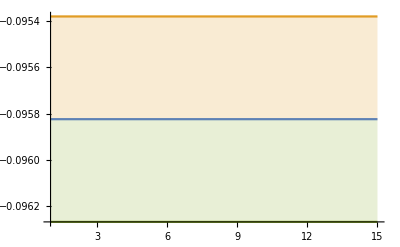

```mathematica
Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,15},Filling->{3->{1},2->{1}}]
```

```mathematica
SpoilHWFLOPlotN3=Show[Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,Length[meanErr2[[5]]]},Filling->{3->{1},2->{1}},PlotRange->{-.2,0}],ListPlot[{Table[{τSteps[[1,i]],meanErr2[[1,i]]},{i,1,Length[meanErr2[[1]]]}],Table[{τSteps[[2,i]],meanErr2[[2,i]]},{i,1,Length[meanErr2[[2]]]}],Table[{τSteps[[3,i]],meanErr2[[3,i]]},{i,1,Length[meanErr2[[3]]]}],Table[{τSteps[[4,i]],meanErr2[[4,i]]},{i,1,Length[meanErr2[[4]]]}],Table[{τSteps[[5,i]],meanErr2[[5,i]]},{i,1,Length[meanErr2[[5]]]}]},PlotRange->{-.1,-0.005},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]],markerlist[[4]],markerlist[[5]]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]},PlotStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau_{\\text{steps}}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3(\\text{NNLO})",Magnification->1.2]]
```

-Graphics-

### a=0.4 dτ=0.2

#### QCD LO - HWF

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={430,430,430,430,430};
NWalkers=200;
Nf4α1LoopBig={0.4,0.4,0.4,0.4,0.4};
aList={1,2,3,4,5};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
csvData=Table[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"],{xx,1,Length[aList]}]
```

({mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.0711111111246, -0.07111111163004843, -0.07111111212585342, -0.07111111064049636, -0.0711111113214579, -0.07111111201172876, -0.07111111237415257, -0.07111111089498913, -0.07111111087918802, -0.07111111040322231, -0.07111111070068896, -0.07111111000948413, -0.07111111081638229, -0.071111110679502, -0.07111111078188646, -0.07111111065962103, -0.07111111084373246, -0.07111111070486374, -0.07111111043588439, -0.07111111157533949, -0.07111110980766308, -0.07111111117883646, -0.07111111071475337, -0.07111111138771826, -0.07111111060716167, -0.07111111086020573, -0.07111111117356453, -0.07111111092661855, -0.07111111129529975, -0.07111111057443072, -0.07111111052900407, -0.07111111162901254, -0.07111111100297839, -0.07111111157260522, -0.07111111136296994, -0.0711111113899789, -0.07111111158418737, -0.07111111072969459, -0.07111111106877237, -0.0711111117453036, -0.07111111224641989, -0.07111111231131804, -0.07111111093395875, -0.07111111167796108, -0.07111111065718158, -0.07111111125064429, -0.0711111108895886, -0.07111111107829837, -0.07111111209482499, -0.07111111124930636, -0.07111111027507001, -0.07111111096758137, -0.07111111049809377, -0.07111111095383561, -0.07111111119627853, -0.07111111093740244, -0.07111111045668629, -0.0711111115648634, -0.07111111050097209, -0.07111111122631246, -0.07111111094610022, -0.07111111111932396, -0.07111111082578274, -0.07111111146825985, -0.07111111122504053, -0.07111111191436226, -0.07111111038758175, -0.07111111095708358, -0.07111111116229368, -0.07111111111026619, -0.07111111277590751, -0.07111111234746821, -0.07111111189573063, -0.07111111135787962, -0.07111111060448712, -0.07111111132007267, -0.07111111086479549, -0.07111111168509593, -0.07111111100363843, -0.07111111113498289, -0.07111111119398685, -0.071111111374229, -0.07111111152529806, -0.0711111117620004, -0.07111111004330141, -0.07111111086460246, -0.0711111115513506, -0.0711111110487482, -0.07111111079821862, -0.0711111102466272, -0.07111111210816046, -0.07111111062897191, -0.07111111040569826, -0.07111111218934983, -0.0711111109259393, -0.07111111126132343, -0.07111111115961193, -0.07111111109010375, -0.0711111112434996, -0.07111111195702906, -0.07111111014782985, -0.07111111102334622, -0.07111111157401952, -0.07111111015113185, -0.07111111150850702, -0.07111111046031413, -0.07111111140707504, -0.07111111084268194, -0.07111111050373152, -0.0711111107231823, -0.07111111132572866, -0.07111111127158508, -0.07111111143931029, -0.07111111089669692, -0.07111111076503253, -0.07111111119866025, -0.07111111063700798, -0.07111111060840992, -0.0711111119117551, -0.07111110962327664, -0.07111111150439035, -0.0711111096645365, -0.0711111110878069, -0.07111111072138959, -0.07111111082379307, -0.07111111050347953, -0.07111111075157547, -0.07111111138837563, -0.0711111106767776, -0.07111111071413768, -0.07111111145476318, -0.07111111066406696, -0.07111111186657246, -0.07111111206384636, -0.07111111139465887, -0.07111111094474849, -0.07111111030441361, -0.07111111084688142, -0.07111111114701212, -0.07111111122815715, -0.07111111053410202, -0.07111111098537032, -0.07111111060279492, -0.07111111061125297, -0.0711111115524145, -0.07111111029798184, -0.07111111166596389, -0.07111111100231288, -0.07111111090159333, -0.07111111160070359, -0.07111111074315328, -0.07111111120409719, -0.07111111052570067, -0.07111111176881557, -0.0711111104991265, -0.07111111121047019, -0.07111111133830034, -0.0711111110479827, -0.07111111033610258, -0.0711111109902381, -0.07111111056963218, -0.07111111128102776, -0.07111111326085344, -0.07111111090604326, -0.07111111136105232, -0.0711111102305221, -0.07111111186479087, -0.07111111018661541, -0.0711111109838665, -0.07111111152903761, -0.07111111062317371, -0.07111111085274088, -0.0711111113406613, -0.07111111149514035, -0.07111111247928668, -0.0711111108062271, -0.07111111070173262, -0.07111111175493395, -0.07111111141097975, -0.07111111127924881, -0.07111111138640244, -0.0711111112794679, -0.07111111119624487, -0.07111111157623945, -0.07111111115468285, -0.0711111110975385, -0.0711111112727544, -0.07111111169396696, -0.07111111021109111, -0.07111111111538705, -0.0711111107427481, -0.07111111131116414, -0.0711111104523713, -0.07111111106422151, -0.0711111114846196, -0.07111111083701872, -0.07111111256318763, -0.07111111149585651, -0.07111111106020832, -0.07111111171570163, -0.07111111097128218, -0.07111111150626144, -0.07111111051168874, -0.0711111117266046, -0.07111111190812039, -0.07111111124340005, -0.07111111147576095, -0.07111111066571843, -0.07111111130951243, -0.07111111146493009, -0.07111111140528223, -0.0711111111116683, -0.07111111017098107, -0.07111111056778469, -0.07111112157118733, -0.07111111300336301, -0.07111111300701962, -0.0711111115023771, -0.07111110956199476, -0.0711111114708563, -0.07111111317278837, -0.07111111246136582, -0.07111111153809234, -0.07111111013695795, -0.07111111024233134, -0.07111111030421487, -0.07111111157153868, -0.07111111063730527, -0.07111111213070968, -0.07111111101470653, -0.07111110819076728, -0.07111111238395065, -0.0711111102388169, -0.07111111205323789, -0.07111111150275556, -0.07111111160643784, -0.07111111147178166, -0.07111111129735037, -0.07111111180678788, -0.07111111085399802, -0.07111111220618739, -0.07111110948347822, -0.07111111071764217, -0.07111111174409526, -0.07111111238161107, -0.07111111048330937, -0.07111111158198054, -0.07111111104436812, -0.07111111099365648, -0.07111111146291467, -0.07111111190748122, -0.0711111109086709, -0.07111111106241762, -0.07111111092921335, -0.07111111049294964, -0.07111110992604527, -0.07111111255913363, -0.07111111190369028, -0.07111111006437607, -0.07111111178395092, -0.07111111245684873, -0.07111111185460403, -0.07111111105586385, -0.07111111031047566, -0.07111111088141549, -0.07111111168568693, -0.07111111189800078, -0.07111111152616299, -0.0711111111027292, -0.07111111148105989, -0.07111111080810048, -0.07111111087565963, -0.07111111121687176, -0.07111111028638974, -0.07111111057473272, -0.07111111090607222, -0.07111111047298083, -0.07111110844785232, -0.07111111156566971, -0.07111111099303184, -0.07111111126664962, -0.07111111076081218, -0.07111111084677586, -0.07111111112112986, -0.07111111058960852, -0.07111111260656744, -0.07111111133672376, -0.07111110926645886, -0.0711111111791222, -0.07111111044487965, -0.07111111093808693, -0.07111111018659037, -0.07111111089859218, -0.07111111063735943, -0.07111111035201734, -0.07111111121964295, -0.07111111088605361, -0.07111111119963878, -0.0711111118176018, -0.07111111307057699, -0.07111111023226148, -0.0711111106680031, -0.07111111200805152, -0.07111111163149793, -0.07111111032865955, -0.07111111162226372, -0.07111111114445409, -0.07111111113392647, -0.07111111156122389, -0.07111111163702923, -0.07111111113984979, -0.07111111047149496, -0.07111111164654492, -0.07111111099733192, -0.07111110990158657, -0.07111111103770094, -0.07111111158739666, -0.07111110995147636, -0.0711111120465576, -0.07111111028111543, -0.07111111094405292, -0.07111111185221157, -0.0711111131901115, -0.07111111053769258, -0.07111111149193612, -0.07111111203973622, -0.07111111165585252, -0.07111111170082303, -0.07111111138470773, -0.07111111001384578, -0.07111111224196427, -0.07111111079048132, -0.0711111119447783, -0.07111111070816223, -0.07111111129753364, -0.07111111176133258, -0.0711111115760663, -0.07111111018323187, -0.07111111056044139, -0.07111111161493368, -0.07111111139487068, -0.07111111045660173, -0.07111111120322094, -0.07111111135690254, -0.07111111050913256, -0.07111111070793055, -0.07111111204442436, -0.07111111056927966, -0.07111111058919097, -0.07111111175188552, -0.07111111154897545, -0.0711111108816124, -0.071111110250283, -0.07111111115891268, -0.07111111117416063, -0.07111111063588936, -0.07111111072490664, -0.0711111114657635, -0.07111111124409494, -0.07111111003762749, -0.07111111108973515, -0.07111111070984451, -0.07111110962449368, -0.07111111038673244, -0.07111111054167264, -0.07111111161017536, -0.07111111057029534, -0.0711111107409547, -0.07111111137541899, -0.07111111135023399, -0.0711111106006579, -0.07111111077195127, -0.07111111144986236, -0.0711111111437857, -0.07111111044280312, -0.07111111043753553, -0.07111111078675066, -0.07111111149096218, -0.07111111124524033, -0.07111111173591121, -0.07111111115033616, -0.07111111035883813, -0.07111111153655675, -0.07111111064371123, -0.07111111070591446, -0.07111111086505213, -0.07111111139519798],[1.3203941378897724e-09, 0.0, 9.336596487408234e-10, 0.0, nan, 9.336596487408234e-10, 1.6171459485960176e-09, 1.3203941378897724e-09, 1.3203941378897724e-09, nan, 9.336596487408234e-10, 0.0, 0.0, 1.3203941378897724e-09, 0.0, 1.6171459485960176e-09, nan, 0.0, 0.0, 0.0, 9.336596487408234e-10, 0.0, 1.6171459485960176e-09, 9.336596487408234e-10, 0.0, 9.336596487408234e-10, 0.0, nan, 9.336596487408234e-10, 0.0, 0.0, nan, 0.0, 1.3203941378897724e-09, 0.0, 9.336596487408234e-10, 0.0, 1.6171459485960176e-09, 0.0, 9.336596487408234e-10, nan, 0.0, 1.3203941378897724e-09, 9.336596487408234e-10, 9.336596487408234e-10, 0.0, 0.0, 9.336596487408234e-10, 1.3203941378897724e-09, nan, 1.3203941378897724e-09, 1.867319297481647e-09, 1.3203941378897724e-09, nan, 0.0, nan, nan, 0.0, 0.0, 0.0, 0.0, 0.0, nan, 0.0, 1.3203941378897724e-09, 9.336596487408234e-10, 0.0, 9.336596487408234e-10, nan, 1.6171459485960176e-09, 1.3203941378897724e-09, 0.0, 0.0, 9.336596487408234e-10, 0.0, nan, 0.0, 0.0, 9.336596487408234e-10, 0.0, nan, 0.0, 1.3203941378897724e-09, 0.0, nan, 0.0, 1.3203941378897724e-09, nan, 1.3203941378897724e-09, 0.0, 1.3203941378897724e-09, 9.336596487408234e-10, 9.336596487408234e-10, nan, nan, 9.336596487408234e-10, 9.336596487408234e-10, 1.6171459485960176e-09, 0.0, 1.3203941378897724e-09, 9.336596487408234e-10, 9.336596487408234e-10, nan, nan, nan, 9.336596487408234e-10, 0.0, 1.3203941378897724e-09, 9.336596487408234e-10, 1.3203941378897724e-09, 9.336596487408234e-10, nan, 9.336596487408234e-10, nan, 1.3203941378897724e-09, 1.3203941378897724e-09, 9.336596487408234e-10, 1.3203941378897724e-09, nan, 9.336596487408234e-10, 1.6171459485960176e-09, 9.336596487408234e-10, 0.0, 9.336596487408234e-10, 9.336596487408234e-10, 1.6171459485960176e-09, nan, nan, 0.0, 0.0, 9.336596487408234e-10, nan, 9.336596487408234e-10, 0.0, 0.0, nan, 0.0, 1.6171459485960176e-09, 9.336596487408234e-10, 9.336596487408234e-10, 0.0, nan, 0.0, 0.0, 0.0, 1.3203941378897724e-09, nan, 1.3203941378897724e-09, 9.336596487408234e-10, 1.3203941378897724e-09, nan, 0.0, 9.336596487408234e-10, 9.336596487408234e-10, nan, nan, 0.0, 0.0, 9.336596487408234e-10, 1.6171459485960176e-09, 0.0, 0.0, 2.286989732841192e-09, 9.336596487408234e-10, nan, 0.0, 1.3203941378897724e-09, 0.0, 9.336596487408234e-10, 9.336596487408234e-10, 0.0, 1.3203941378897724e-09, 9.336596487408234e-10, 9.336596487408234e-10, 9.336596487408234e-10, 9.336596487408234e-10, 0.0, 0.0, 1.3203941378897724e-09, 0.0, 1.3203941378897724e-09, 1.6171459485960176e-09, 0.0, nan, 1.6171459485960176e-09, 9.336596487408234e-10, 9.336596487408234e-10, 1.3203941378897724e-09, nan, 0.0, 1.3203941378897724e-09, 1.3203941378897724e-09, 1.3203941378897724e-09, 1.3203941378897724e-09, 1.867319297481647e-09, 1.3203941378897724e-09, 1.6171459485960176e-09, 0.0, 9.336596487408234e-10, 9.336596487408234e-10, 0.0, 0.0, 9.336596487408234e-10, 9.336596487408234e-10, 9.336596487408234e-10, 1.3203941378897724e-09, 9.336596487408234e-10, nan, 9.336596487408234e-10, nan, 9.336596487408234e-10, 1.3203941378897724e-09, 9.336596487408234e-10, nan, 8.808127509983524e-09, 9.336596487408234e-10, 9.336596487408234e-10, 1.3203941378897724e-09, 9.336596487408234e-10, 9.336596487408234e-10, 1.3203941378897724e-09, 1.3203941378897724e-09, 9.336596487408234e-10, 9.336596487408234e-10, 9.336596487408234e-10, nan, 9.336596487408234e-10, nan, 9.336596487408234e-10, 0.0, 1.6171459485960176e-09, 9.336596487408234e-10, 9.336596487408234e-10, 0.0, nan, 1.3203941378897724e-09, 0.0, 9.336596487408234e-10, nan, 9.336596487408234e-10, 9.336596487408234e-10, nan, 0.0, 0.0, 9.336596487408234e-10, 9.336596487408234e-10, 9.336596487408234e-10, 1.3203941378897724e-09, 9.336596487408234e-10, 9.336596487408234e-10, 0.0, 1.3203941378897724e-09, 0.0, 9.336596487408234e-10, 9.336596487408234e-10, 1.3203941378897724e-09, 9.336596487408234e-10, 0.0, 0.0, 1.3203941378897724e-09, nan, 0.0, 0.0, nan, nan, 0.0, 0.0, 9.336596487408234e-10, 0.0, 9.336596487408234e-10, 9.336596487408234e-10, 9.336596487408234e-10, 0.0, 9.336596487408234e-10, 9.336596487408234e-10, 9.336596487408234e-10, 1.3203941378897724e-09, 1.6171459485960176e-09, 1.867319297481647e-09, 0.0, nan, 0.0, 0.0, nan, 9.336596487408234e-10, 1.3203941378897724e-09, 0.0, 2.087726442433057e-09, 0.0, 0.0, 9.336596487408234e-10, nan, nan, nan, 1.6171459485960176e-09, 9.336596487408234e-10, 1.3203941378897724e-09, 9.336596487408234e-10, 9.336596487408234e-10, 9.336596487408234e-10, 9.336596487408234e-10, nan, 1.867319297481647e-09, 0.0, 1.3203941378897724e-09, 9.336596487408234e-10, 0.0, nan, nan, 0.0, 1.3203941378897724e-09, 9.336596487408234e-10, 9.336596487408234e-10, 0.0, 1.6171459485960176e-09, 0.0, 0.0, nan, 9.336596487408234e-10, 3.849577350135498e-09, 1.3203941378897724e-09, 1.3203941378897724e-09, 1.6171459485960176e-09, 9.336596487408234e-10, 9.336596487408234e-10, 1.3203941378897724e-09, 0.0, 9.336596487408234e-10, 9.336596487408234e-10, 1.6171459485960176e-09, 1.3203941378897724e-09, nan, nan, 9.336596487408234e-10, 1.3203941378897724e-09, 9.336596487408234e-10, 0.0, 9.336596487408234e-10, 0.0, nan, 0.0, 9.336596487408234e-10, 9.336596487408234e-10, 9.336596487408234e-10, 0.0, nan, 0.0, nan, 0.0, 9.336596487408234e-10, 1.3203941378897724e-09, nan, 1.3203941378897724e-09, 0.0, 1.3203941378897724e-09, nan, 0.0, 9.336596487408234e-10, nan, 0.0, 9.336596487408234e-10, nan, 1.867319297481647e-09, 1.3203941378897724e-09, nan, nan, nan, 1.3203941378897724e-09, 0.0, 0.0, 0.0, 0.0, 9.336596487408234e-10, 0.0, 0.0, 9.336596487408234e-10, 9.336596487408234e-10, nan, nan, nan, 1.3203941378897724e-09, 0.0, nan, 9.336596487408234e-10, nan, 1.3203941378897724e-09, nan],-0.0711111,nan,0.0318529}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.05647342864762567, -0.05811050026126443, -0.06075727449313358, -0.05960856076907892, -0.058036410023579836, -0.05905609559329726, -0.06251930060247962, -0.05695647438576396, -0.057373481689484994, -0.05808878496914413, -0.0557247496579528, -0.0567070429135055, -0.05822876158672041, -0.057520066436267676, -0.058194659286285984, -0.05871829513535229, -0.06022735955422612, -0.05848277767540934, -0.058510277011128195, -0.05989188674966702, -0.061486060488909366, -0.05944927417282053, -0.061134385307556265, -0.06142827117920198, -0.061083134698198566, -0.058260023936481393, -0.058471733198128574, -0.057288855593203514, -0.05778228121608832, -0.05746685567478672, -0.059340429561038285, -0.05759305412791851, -0.0567430377125693, -0.056454802243460965, -0.056582410868670836, -0.05736740225794815, -0.05666562454860208, -0.05516216619624058, -0.05567415417777217, -0.054993435571536, -0.054922833823526925, -0.054493386132297726, -0.05475019492831962, -0.05525219583486076, -0.05463266678333578, -0.0550088492033282, -0.05637496057891573, -0.05466635159893766, -0.054854380919700865, -0.062117614331113936, -0.06087919705556648, -0.058847580894514084, -0.05841931567013647, -0.05918004239209619, -0.05832840541474548, -0.059372484112751214, -0.059906617436278, -0.06067439034032717, -0.059426779930679165, -0.06072675382568152, -0.0597586323993031, -0.060332645137466306, -0.05935318686001561, -0.05863509555019708, -0.06013794134172885, -0.05834805901422773, -0.06189192203820071, -0.06402377807434138, -0.06768394461622554, -0.06461354480947379, -0.06169225024603517, -0.06309426379055182, -0.06193971852402141, -0.06256451143446055, -0.06399858745885774, -0.060208099197372224, -0.06070835831858915, -0.06127833262585637, -0.061359445345726064, -0.06364277980483847, -0.06208940754171052, -0.061796913378389925, -0.06300033505037594, -0.06701668184046851, -0.060729249943407906, -0.06237471323694675, -0.06304940799050053, -0.06683760810379365, -0.06873127830109929, -0.06658623437625404, -0.06860960168414847, -0.06442079965305249, -0.06371390312089918, -0.06729639590346889, -0.0663805346576122, -0.06372319456867714, -0.06462134043259785, -0.06425297184861771, -0.06650394096783478, -0.06522037792141307, -0.06284599394156264, -0.06405189451240026, -0.06461390917404725, -0.0625300804213193, -0.06235062389550834, -0.0664941349891191, -0.06561944515333952, -0.06723807525478219, -0.06470461619910979, -0.06800793907959377, -0.06575478341188895, -0.06267407259805445, -0.06747616510685056, -0.06594910610161372, -0.062149050832939, -0.06482076740510952, -0.06916479501152223, -0.07284628185767761, -0.06548365240003087, -0.06734537368627329, -0.06970247135625714, -0.06882948383082199, -0.07045765777146429, -0.06994771242301519, -0.07109231626283083, -0.07097738474708498, -0.07485178915563337, -0.07296131645285928, -0.06959842264842764, -0.07499253000768194, -0.22884356137985415, -0.08743599250230191, -0.07436808687256179, -0.08949142641730078, -0.07428548590261248, -0.08323960858443837, -0.08200229888119198, -0.07172791917347167, -0.07244601314191883, -0.06936566430910217, -0.07163061351847173, -0.06829499401164695, -0.06601947913395882, -0.07046091442719135, -0.06700685518000049, -0.06481303258965793, -0.06396211745146375, -0.06244189084952229, -0.06364581660786242, -0.06327027730393836, -0.061374689352297306, -0.06123632425844901, -0.05900498043554143, -0.05701274521059542, -0.0591422189390454, -0.06021414769005178, -0.06117537608171305, -0.058822551735658285, -0.06297999297502213, -0.06153374316396967, -0.0578630037125982, -0.058000214402890764, -0.05663061754443568, -0.05668185889939778, -0.05663263509982456, -0.05715133554570027, -0.05693653481139757, -0.055898549598681735, -0.056499033276947414, -0.055998038985039585, -0.05578023963500223, -0.05529655186714362, -0.05557839947004247, -0.055987592101175175, -0.05665920283222088, -0.055957062767939936, -0.05545441182030983, -0.05591491315334953, -0.05837476832466982, -0.059534408340739885, -0.06279543849909142, -0.05822810599344766, -0.05776518478549339, -0.05901135160427828, -0.05843128558924155, -0.05879173282064476, -0.059180537582695265, -0.06118904706838573, -0.061158118080896905, -0.06571899186241274, -0.06841128430683527, -0.06359514883329534, -0.06235624679383978, -0.06094086233110022, -0.0613077556798913, -0.05877745583844881, -0.058725167937826644, -0.0586661579743013, -0.06086404171421163, -0.05876432994676199, -0.060429295355491665, -0.06227520693434549, -0.061726622953618686, -0.06743988514405312, -0.08388869981809693, -0.06679534358983713, -0.0715772937326054, -0.070284698125178, -0.07073227699476135, -0.06908863439725986, -0.06744328154762873, -0.07033519803639411, -0.07249218493175073, -0.07591071603847505, -0.07696694860599823, -0.07484621441888192, -0.0726032060108288, -0.0680802856764006, -0.0673767647277064, -0.07855697632683918, -0.07625781769593401, -0.07102958287049894, -0.07344013287173985, -0.0707639772671856, -0.07245170846827237, -0.07652042786585568, -0.07638871536006757, -0.0718019796112175, -0.06868885801029383, -0.0690357435533157, -0.067273962156469, -0.0667287706419905, -0.06657665633462813, -0.06655172291862944, -0.06522669686730279, -0.06845016666549247, -0.0667409932949483, -0.06864577101494215, -0.07157119841235536, -0.0749686763321491, -0.07583312124505408, -0.0694972280016489, -0.07197931975055122, -0.07071574733293924, -0.06934085650332861, -0.07296434591558862, -0.07614029584535366, -0.0703235448208804, -0.06677927613469556, -0.06455651406559089, -0.06472800479575827, -0.06707039222287005, -0.06559112685911923, -0.0620635888267292, -0.061305950958519005, -0.06304324531262424, -0.0651640122873852, -0.06348775511472789, -0.06621500208691765, -0.06519096361755784, -0.06858906053486546, -0.06825534773458146, -0.06815628446021058, -0.06758329902676274, -0.06620874661377026, -0.0652179730697309, -0.06422105735427514, -0.06789940267412323, -0.06620537105750623, -0.06501559737314952, -0.06415092638101925, -0.06632818810350444, -0.0638911635085093, -0.06357432049534387, -0.06426772093750951, -0.06555074571710137, -0.06427827212439662, -0.06307451979525809, -0.06237086384821314, -0.06280268845497958, -0.06636951696831413, -0.0643333108455861, -0.0694434455188244, -0.07102569639797678, -0.07618677376355693, -0.07260310429687754, -0.09661101450960087, -0.07389375956823185, -0.07670322844431912, -0.07933337853367055, -0.07901284420798498, -0.0777284271425965, -0.08279852604207906, -0.08055451348217438, -0.07574301138414657, -0.07882577912648285, -0.07819241077056462, -0.07731414662716038, -0.08708439815098591, -0.09692777410903457, -0.08681524431202602, -0.0860263633901966, -0.08258336507478985, -0.0859689121004706, -0.07970051385863867, -0.07525091829727645, -0.07587665237656943, -0.07932571245378987, -0.07544033246530711, -0.08361093938010823, -0.10235826347546162, -0.08460445463845602, -0.08417328219984885, -0.08352886150933299, -0.08727996304980591, -0.08709378930037907, -0.08114176317617004, -0.08591817097851885, -0.08291319193233673, -0.09301685558573972, -0.0836291654627763, -0.07705992072778832, -0.07833102617332723, -0.08264554060097795, -0.08688251428777129, -0.08104737140172308, -0.07517737550363893, -0.07899198191503866, -0.0783051275416191, -0.07442175994722218, -0.07744443533040528, -0.08952428350267008, -0.10410667017858899, -0.08408213839415613, -0.08172044389950323, -0.09276866599304623, -0.08915631127799148, -0.09093724697355593, -0.07958431692974739, -0.07747292038744934, -0.07327493939143148, -0.08605557643862861, -0.0808736377809982, -0.1076294820387117, -0.08376025926398409, -0.09826852914600274, -0.08465598149187954, -0.08008619579625584, -0.09815490210322624, -0.07963605756218052, -0.0720681528413471, -0.07273892655289411, -0.07095675093138286, -0.06736920737276716, -0.06761422286288393, -0.06428882363774972, -0.06249915787875351, -0.06275372071506082, -0.06701282448947325, -0.06900844328910131, -0.06584975148809667, -0.07197697392463004, -0.0661797524358836, -0.06498636604739712, -0.061433327269867326, -0.061436561364426094, -0.059647611272113536, -0.062362139792397644, -0.06320595795573572, -0.0629362768445784, -0.0642471561865446, -0.06817126405978362, -0.08207374506116044, -0.08377431165461606, -0.0892303694039679, -0.07793943178532774, -0.07997991211118585, -0.07868829598898301, -0.09461569764833082, -0.07894458967298275, -0.07344861574180106, -0.07353610188902354, -0.08500385384723821, -0.07086372595925015, -0.07710701141403895, -0.08672141356223351, -0.08179297243252207],[0.002829888388391662, 0.0034885281460672363, 0.004111761629550064, 0.0034050357322465887, 0.002801486278383683, 0.0035480368812049125, 0.006384888521100113, 0.0027803282729859887, 0.0028527343485453133, 0.003494210202987805, 0.002347693140973878, 0.0023742782947494367, 0.0030581364022297373, 0.002743127223834062, 0.002977108891957309, 0.0036026705308128473, 0.003608936582335198, 0.0030444745936199897, 0.0025762139918573397, 0.0036767623772786355, 0.004167583761244591, 0.003181908392882362, 0.004259533164622723, 0.004259088348102453, 0.004067472731948417, 0.002721007517543172, 0.0030775638442442944, 0.0023597308407374965, 0.0028549055971295607, 0.002168179793932683, 0.0031263189067807116, 0.002257813575263347, 0.0019317214216373272, 0.0019401052907752243, 0.0019941834376659582, 0.0022010607010269803, 0.002119590341067784, 0.001939909956819161, 0.002040726198885687, 0.0018166299409075786, 0.0019375307608871623, 0.0018958170102731662, 0.002022512391016708, 0.0027682981344580014, 0.002060502480248464, 0.002043124237825536, 0.0029239165523407408, 0.0020909819232887606, 0.002254555844449909, 0.006688949968715726, 0.00550766706021472, 0.0033654778155188378, 0.0026715433077715337, 0.0029253921641391348, 0.002518500090388743, 0.002662378296157557, 0.003134129877569158, 0.0029485347271378717, 0.0026634371248470384, 0.003006702577307372, 0.0029453883113023304, 0.0030339365643867874, 0.003016589805581927, 0.0030742198064500218, 0.0037333233575483483, 0.002728584097976075, 0.005698634282663392, 0.0074193979268761074, 0.008461214563046906, 0.006326300333543682, 0.003912016884380612, 0.004325591669588612, 0.0034033105732608018, 0.0035901672792305957, 0.004498024854267073, 0.0030958782920807375, 0.0031534264106561002, 0.00315889505559059, 0.003182759968383187, 0.00548341968273451, 0.003445729321499898, 0.003229357927581597, 0.004774956425916939, 0.007165850578676234, 0.0027452177153888266, 0.0035897413948627367, 0.0032457249572114054, 0.005037426867589117, 0.005816804731076579, 0.0057731350597233924, 0.008423668080401753, 0.004535738492556047, 0.004213205595561546, 0.006157189225357721, 0.005544819479462879, 0.0034425889428476267, 0.004005209678921956, 0.0036189404924498367, 0.0038494868880170397, 0.00400535030510902, 0.003194939714801103, 0.003817188928999698, 0.0042838151309729225, 0.0029789530181330093, 0.0029102650582617244, 0.00471244687296609, 0.004609795599186091, 0.006452665769294314, 0.004766599846400463, 0.007036728353375377, 0.006294677241433052, 0.004345080236373256, 0.006957364557373647, 0.006649862072194659, 0.0029619704982103527, 0.004810172107131642, 0.008568339198466661, 0.009171606137337428, 0.004481910207959558, 0.006604104594519012, 0.006982795716642448, 0.005967904107350447, 0.006878822353584464, 0.006851024229707794, 0.006750721135904558, 0.0069525145379995415, 0.008455672780595922, 0.00703691885284083, 0.005278789647757077, 0.007125693326467372, 0.14495565453526482, 0.013783671859317522, 0.007025133045785383, 0.01895944948047501, 0.007580241527057582, 0.011070934318212712, 0.011286064779848141, 0.005970792503592899, 0.006480314804179261, 0.005074481509651362, 0.006420677744674162, 0.005632696491521874, 0.0037780075116561887, 0.006843558859398356, 0.003980937959582456, 0.003968063623907539, 0.002906934094049234, 0.0027249124204686216, 0.003270145544972016, 0.0035556343971895714, 0.0032527880445305745, 0.003653137294781457, 0.0026767282064562546, 0.0019009115070855365, 0.0026998415446996896, 0.0040088977481510845, 0.0044651585365398615, 0.0027242749727772915, 0.005407315435368143, 0.004377066149888087, 0.002764764124909441, 0.002673709516224539, 0.0023307154920371356, 0.0020309333423344338, 0.0019405050652932852, 0.0021147999353969232, 0.00205411468904628, 0.0019036684787214666, 0.0022613445470343685, 0.001954513455397295, 0.0018709239904651823, 0.0018277279400358182, 0.0019096346137588709, 0.002181471365195687, 0.0023942078612955294, 0.0025412651748136453, 0.0023627321326832153, 0.0028292542509563818, 0.004010219244745305, 0.004349753804514056, 0.006499295475891078, 0.00425088027377647, 0.0033992704541391475, 0.004062181782346103, 0.00374864382409064, 0.003692353080612383, 0.0037478637926685004, 0.0048719893665258645, 0.0046761551162360524, 0.008578399475367239, 0.00780594674438405, 0.005150489820113383, 0.0049466734002267315, 0.003934406307504274, 0.003934489999518134, 0.0033809401210446177, 0.0034155885119717157, 0.003527611190384674, 0.0039341000838160126, 0.00311236216695667, 0.003720005083305199, 0.004587780335104727, 0.004275993725894993, 0.005910068171681487, 0.02156622557376825, 0.005323686514624804, 0.00612890094656993, 0.005716960457896962, 0.006198860022180806, 0.00535026005460558, 0.005577587107683211, 0.006130957857051896, 0.006607977695292654, 0.007277634665762596, 0.0070184300792373484, 0.006190159045463856, 0.00570187026239387, 0.004569626787439312, 0.004418128086429492, 0.010634180079239799, 0.009040047006988555, 0.005385787786096125, 0.00837326943129623, 0.0074659285416008745, 0.007898191815473231, 0.008754479924624891, 0.008038208026406507, 0.0062782576825456, 0.004268385311674346, 0.0045395116844471825, 0.004210264648859409, 0.004202486279800689, 0.004160939553035511, 0.004865276763631358, 0.004949528375006545, 0.005969339837303209, 0.0057058118023193445, 0.006257106741706451, 0.0074646580541077295, 0.011102432907387659, 0.013169124801824446, 0.007838179267373487, 0.008823411593318158, 0.007622050794654304, 0.0062483646743034076, 0.010142580988278032, 0.010167729045514011, 0.006216057265417542, 0.004246926389490982, 0.0031149609239425496, 0.003344274621842941, 0.004098187956300484, 0.0037434528463849356, 0.002679016168617091, 0.0027064315515152025, 0.0030326084638106227, 0.0035126798311496616, 0.0035689950138758308, 0.004336306737021672, 0.0032167775783665904, 0.00459093128268279, 0.004164934571272794, 0.004810798751403584, 0.00444151077758602, 0.004287597968198426, 0.003521851545724983, 0.003096941405578811, 0.005313507606344349, 0.0033919028212821, 0.002814300273705019, 0.0024911445725599992, 0.0034257189717304, 0.002835676174901402, 0.0028827442518529894, 0.0032414368365589435, 0.004098123955770345, 0.003931203916812357, 0.0032863686347733073, 0.0031572910662431204, 0.003707403356281866, 0.00515461783622714, 0.004016532413067082, 0.006734209697446466, 0.006884321434455129, 0.00877345045686484, 0.00691484954203454, 0.02774155314416258, 0.0078002281408293146, 0.008221876455666311, 0.009403566065566185, 0.00792472684269534, 0.0072513743448138135, 0.010408468519428228, 0.010044307203110617, 0.006914890312947242, 0.007714148547199343, 0.007242761700587174, 0.007124599132939067, 0.010486554327240653, 0.01620006037392387, 0.010603241117966932, 0.009511569299442892, 0.008625507643090368, 0.011776454217214991, 0.008511839680260367, 0.006804223529468587, 0.0070534350154949485, 0.008533603717396455, 0.007608232514604663, 0.010951594397407371, 0.02123607699197448, 0.011126490199420695, 0.01025479690878696, 0.010806389705997102, 0.012967455052227055, 0.00998182055821712, 0.008024347283933298, 0.01062718446247538, 0.008843110034319025, 0.015918214843384473, 0.0072225133428461125, 0.004350029398038628, 0.005580314982163072, 0.009065598896655125, 0.013591839770620954, 0.009410773635793282, 0.0058285309762093574, 0.007874639148805145, 0.006847300772642242, 0.005508504204152607, 0.006796442686621733, 0.014131174067500769, 0.02544522139785611, 0.01047524155485862, 0.009468812596092354, 0.01449700979914058, 0.01072838258665115, 0.01206402682116788, 0.006292662954868221, 0.008852513545790914, 0.0050296508952177976, 0.016152444350633767, 0.012138452035588347, 0.03673675459071305, 0.01152360810495946, 0.01988644967948383, 0.008821526630791783, 0.006940608775335733, 0.02057441658378168, 0.009384027232689522, 0.005317185724379958, 0.005586007762740584, 0.005056253420590178, 0.004140788728001273, 0.0048072747645924695, 0.003824808979817001, 0.0033698248738294224, 0.0042369801808007646, 0.007753076626868341, 0.009234918711639773, 0.006251734912008963, 0.01065305242487425, 0.005445528713493101, 0.0047934185913756045, 0.003623867121851526, 0.0031010137462162933, 0.0026683712697384235, 0.004228001482379519, 0.004383621164493537, 0.004321486867887549, 0.004478017413626964, 0.007488151887063549, 0.016256503322606197, 0.016187482599455447, 0.01770026801748302, 0.012379020291760943, 0.013656316373071372, 0.013689935004316355, 0.030255384368567305, 0.014790882697739503, 0.009964776777671052, 0.009272252033927775, 0.016562443682354454, 0.008781805393430837, 0.01207202161178146, 0.019649160642559015, 0.01602178777269097],-0.0565596,0.000481723,0.930993}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.061852502968504745, -0.06511937414653969, -0.06133077530821133, -0.09221833999622295, -0.08926331275631559, -0.07600973769604086, -0.059384781954468724],[0.007356872902153714, 0.009712195798931287, 0.01090662941887267, 0.033600085433575365, 0.03192370430599218, 0.020509672852772835, 0.007866879137414894],-0.0473418,0.00233788,1.17932}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.04939020715418703, -0.04516502363778605, -0.04549055309547252, -0.04676868223521018, -0.04619938822770984, -0.0477086424154278, -0.04949920313528945, -0.04969019994120415, -0.04815039767049233, -0.045059377169868395, -0.04489820098449318, -0.04476515118501876, -0.04566798707588408],[0.0038864230288285576, 0.0028424832689307542, 0.003183099150078028, 0.003898924284635121, 0.0034741725289661584, 0.0043260833418886395, 0.004596198962212853, 0.006432134936864126, 0.005232450807243538, 0.0032746481027451494, 0.004406336291995058, 0.004698548170489575, 0.004744983361342102],-0.0441722,0.000842997,0.522922}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.07419263025786949, -0.13617041564538504, -0.05639433853497755, -0.06655398813831434, -0.04904690855214516, -0.050303877580226704],[0.021990183443957416, 0.04957828899896384, 0.01133958787038369, 0.015353483103207647, 0.007244772075777169, 0.009988651237884363],-0.0334876,0.0112405,0.622603})

```mathematica
meanErr=Table[Table[csvData[[xx,2,yy]]//StringSplit[#,{",","[","]"}]&,{yy,1,2}],{xx,1,Length[aList]}]
```

({-0.0711111111246, -0.07111111163004843, -0.07111111212585342, -0.07111111064049636, -0.0711111113214579, -0.07111111201172876, -0.07111111237415257, -0.07111111089498913, -0.07111111087918802, -0.07111111040322231, -0.07111111070068896, -0.07111111000948413, -0.07111111081638229, -0.071111110679502, -0.07111111078188646, -0.07111111065962103, -0.07111111084373246, -0.07111111070486374, -0.07111111043588439, -0.07111111157533949, -0.07111110980766308, -0.07111111117883646, -0.07111111071475337, -0.07111111138771826, -0.07111111060716167, -0.07111111086020573, -0.07111111117356453, -0.07111111092661855, -0.07111111129529975, -0.07111111057443072, -0.07111111052900407, -0.07111111162901254, -0.07111111100297839, -0.07111111157260522, -0.07111111136296994, -0.0711111113899789, -0.07111111158418737, -0.07111111072969459, -0.07111111106877237, -0.0711111117453036, -0.07111111224641989, -0.07111111231131804, -0.07111111093395875, -0.07111111167796108, -0.07111111065718158, -0.07111111125064429, -0.0711111108895886, -0.07111111107829837, -0.07111111209482499, -0.07111111124930636, -0.07111111027507001, -0.07111111096758137, -0.07111111049809377, -0.07111111095383561, -0.07111111119627853, -0.07111111093740244, -0.07111111045668629, -0.0711111115648634, -0.07111111050097209, -0.07111111122631246, -0.07111111094610022, -0.07111111111932396, -0.07111111082578274, -0.07111111146825985, -0.07111111122504053, -0.07111111191436226, -0.07111111038758175, -0.07111111095708358, -0.07111111116229368, -0.07111111111026619, -0.07111111277590751, -0.07111111234746821, -0.07111111189573063, -0.07111111135787962, -0.07111111060448712, -0.07111111132007267, -0.07111111086479549, -0.07111111168509593, -0.07111111100363843, -0.07111111113498289, -0.07111111119398685, -0.071111111374229, -0.07111111152529806, -0.0711111117620004, -0.07111111004330141, -0.07111111086460246, -0.0711111115513506, -0.0711111110487482, -0.07111111079821862, -0.0711111102466272, -0.07111111210816046, -0.07111111062897191, -0.07111111040569826, -0.07111111218934983, -0.0711111109259393, -0.07111111126132343, -0.07111111115961193, -0.07111111109010375, -0.0711111112434996, -0.07111111195702906, -0.07111111014782985, -0.07111111102334622, -0.07111111157401952, -0.07111111015113185, -0.07111111150850702, -0.07111111046031413, -0.07111111140707504, -0.07111111084268194, -0.07111111050373152, -0.0711111107231823, -0.07111111132572866, -0.07111111127158508, -0.07111111143931029, -0.07111111089669692, -0.07111111076503253, -0.07111111119866025, -0.07111111063700798, -0.07111111060840992, -0.0711111119117551, -0.07111110962327664, -0.07111111150439035, -0.0711111096645365, -0.0711111110878069, -0.07111111072138959, -0.07111111082379307, -0.07111111050347953, -0.07111111075157547, -0.07111111138837563, -0.0711111106767776, -0.07111111071413768, -0.07111111145476318, -0.07111111066406696, -0.07111111186657246, -0.07111111206384636, -0.07111111139465887, -0.07111111094474849, -0.07111111030441361, -0.07111111084688142, -0.07111111114701212, -0.07111111122815715, -0.07111111053410202, -0.07111111098537032, -0.07111111060279492, -0.07111111061125297, -0.0711111115524145, -0.07111111029798184, -0.07111111166596389, -0.07111111100231288, -0.07111111090159333, -0.07111111160070359, -0.07111111074315328, -0.07111111120409719, -0.07111111052570067, -0.07111111176881557, -0.0711111104991265, -0.07111111121047019, -0.07111111133830034, -0.0711111110479827, -0.07111111033610258, -0.0711111109902381, -0.07111111056963218, -0.07111111128102776, -0.07111111326085344, -0.07111111090604326, -0.07111111136105232, -0.0711111102305221, -0.07111111186479087, -0.07111111018661541, -0.0711111109838665, -0.07111111152903761, -0.07111111062317371, -0.07111111085274088, -0.0711111113406613, -0.07111111149514035, -0.07111111247928668, -0.0711111108062271, -0.07111111070173262, -0.07111111175493395, -0.07111111141097975, -0.07111111127924881, -0.07111111138640244, -0.0711111112794679, -0.07111111119624487, -0.07111111157623945, -0.07111111115468285, -0.0711111110975385, -0.0711111112727544, -0.07111111169396696, -0.07111111021109111, -0.07111111111538705, -0.0711111107427481, -0.07111111131116414, -0.0711111104523713, -0.07111111106422151, -0.0711111114846196, -0.07111111083701872, -0.07111111256318763, -0.07111111149585651, -0.07111111106020832, -0.07111111171570163, -0.07111111097128218, -0.07111111150626144, -0.07111111051168874, -0.0711111117266046, -0.07111111190812039, -0.07111111124340005, -0.07111111147576095, -0.07111111066571843, -0.07111111130951243, -0.07111111146493009, -0.07111111140528223, -0.0711111111116683, -0.07111111017098107, -0.07111111056778469, -0.07111112157118733, -0.07111111300336301, -0.07111111300701962, -0.0711111115023771, -0.07111110956199476, -0.0711111114708563, -0.07111111317278837, -0.07111111246136582, -0.07111111153809234, -0.07111111013695795, -0.07111111024233134, -0.07111111030421487, -0.07111111157153868, -0.07111111063730527, -0.07111111213070968, -0.07111111101470653, -0.07111110819076728, -0.07111111238395065, -0.0711111102388169, -0.07111111205323789, -0.07111111150275556, -0.07111111160643784, -0.07111111147178166, -0.07111111129735037, -0.07111111180678788, -0.07111111085399802, -0.07111111220618739, -0.07111110948347822, -0.07111111071764217, -0.07111111174409526, -0.07111111238161107, -0.07111111048330937, -0.07111111158198054, -0.07111111104436812, -0.07111111099365648, -0.07111111146291467, -0.07111111190748122, -0.0711111109086709, -0.07111111106241762, -0.07111111092921335, -0.07111111049294964, -0.07111110992604527, -0.07111111255913363, -0.07111111190369028, -0.07111111006437607, -0.07111111178395092, -0.07111111245684873, -0.07111111185460403, -0.07111111105586385, -0.07111111031047566, -0.07111111088141549, -0.07111111168568693, -0.07111111189800078, -0.07111111152616299, -0.0711111111027292, -0.07111111148105989, -0.07111111080810048, -0.07111111087565963, -0.07111111121687176, -0.07111111028638974, -0.07111111057473272, -0.07111111090607222, -0.07111111047298083, -0.07111110844785232, -0.07111111156566971, -0.07111111099303184, -0.07111111126664962, -0.07111111076081218, -0.07111111084677586, -0.07111111112112986, -0.07111111058960852, -0.07111111260656744, -0.07111111133672376, -0.07111110926645886, -0.0711111111791222, -0.07111111044487965, -0.07111111093808693, -0.07111111018659037, -0.07111111089859218, -0.07111111063735943, -0.07111111035201734, -0.07111111121964295, -0.07111111088605361, -0.07111111119963878, -0.0711111118176018, -0.07111111307057699, -0.07111111023226148, -0.0711111106680031, -0.07111111200805152, -0.07111111163149793, -0.07111111032865955, -0.07111111162226372, -0.07111111114445409, -0.07111111113392647, -0.07111111156122389, -0.07111111163702923, -0.07111111113984979, -0.07111111047149496, -0.07111111164654492, -0.07111111099733192, -0.07111110990158657, -0.07111111103770094, -0.07111111158739666, -0.07111110995147636, -0.0711111120465576, -0.07111111028111543, -0.07111111094405292, -0.07111111185221157, -0.0711111131901115, -0.07111111053769258, -0.07111111149193612, -0.07111111203973622, -0.07111111165585252, -0.07111111170082303, -0.07111111138470773, -0.07111111001384578, -0.07111111224196427, -0.07111111079048132, -0.0711111119447783, -0.07111111070816223, -0.07111111129753364, -0.07111111176133258, -0.0711111115760663, -0.07111111018323187, -0.07111111056044139, -0.07111111161493368, -0.07111111139487068, -0.07111111045660173, -0.07111111120322094, -0.07111111135690254, -0.07111111050913256, -0.07111111070793055, -0.07111111204442436, -0.07111111056927966, -0.07111111058919097, -0.07111111175188552, -0.07111111154897545, -0.0711111108816124, -0.071111110250283, -0.07111111115891268, -0.07111111117416063, -0.07111111063588936, -0.07111111072490664, -0.0711111114657635, -0.07111111124409494, -0.07111111003762749, -0.07111111108973515, -0.07111111070984451, -0.07111110962449368, -0.07111111038673244, -0.07111111054167264, -0.07111111161017536, -0.07111111057029534, -0.0711111107409547, -0.07111111137541899, -0.07111111135023399, -0.0711111106006579, -0.07111111077195127, -0.07111111144986236, -0.0711111111437857, -0.07111111044280312, -0.07111111043753553, -0.07111111078675066, -0.07111111149096218, -0.07111111124524033, -0.07111111173591121, -0.07111111115033616, -0.07111111035883813, -0.07111111153655675, -0.07111111064371123, -0.07111111070591446, -0.07111111086505213, -0.07111111139519798} | {1.3203941378897724e-09, 0.0, 9.336596487408234e-10, 0.0, nan, 9.336596487408234e-10, 1.6171459485960176e-09, 1.3203941378897724e-09, 1.3203941378897724e-09, nan, 9.336596487408234e-10, 0.0, 0.0, 1.3203941378897724e-09, 0.0, 1.6171459485960176e-09, nan, 0.0, 0.0, 0.0, 9.336596487408234e-10, 0.0, 1.6171459485960176e-09, 9.336596487408234e-10, 0.0, 9.336596487408234e-10, 0.0, nan, 9.336596487408234e-10, 0.0, 0.0, nan, 0.0, 1.3203941378897724e-09, 0.0, 9.336596487408234e-10, 0.0, 1.6171459485960176e-09, 0.0, 9.336596487408234e-10, nan, 0.0, 1.3203941378897724e-09, 9.336596487408234e-10, 9.336596487408234e-10, 0.0, 0.0, 9.336596487408234e-10, 1.3203941378897724e-09, nan, 1.3203941378897724e-09, 1.867319297481647e-09, 1.3203941378897724e-09, nan, 0.0, nan, nan, 0.0, 0.0, 0.0, 0.0, 0.0, nan, 0.0, 1.3203941378897724e-09, 9.336596487408234e-10, 0.0, 9.336596487408234e-10, nan, 1.6171459485960176e-09, 1.3203941378897724e-09, 0.0, 0.0, 9.336596487408234e-10, 0.0, nan, 0.0, 0.0, 9.336596487408234e-10, 0.0, nan, 0.0, 1.3203941378897724e-09, 0.0, nan, 0.0, 1.3203941378897724e-09, nan, 1.3203941378897724e-09, 0.0, 1.3203941378897724e-09, 9.336596487408234e-10, 9.336596487408234e-10, nan, nan, 9.336596487408234e-10, 9.336596487408234e-10, 1.6171459485960176e-09, 0.0, 1.3203941378897724e-09, 9.336596487408234e-10, 9.336596487408234e-10, nan, nan, nan, 9.336596487408234e-10, 0.0, 1.3203941378897724e-09, 9.336596487408234e-10, 1.3203941378897724e-09, 9.336596487408234e-10, nan, 9.336596487408234e-10, nan, 1.3203941378897724e-09, 1.3203941378897724e-09, 9.336596487408234e-10, 1.3203941378897724e-09, nan, 9.336596487408234e-10, 1.6171459485960176e-09, 9.336596487408234e-10, 0.0, 9.336596487408234e-10, 9.336596487408234e-10, 1.6171459485960176e-09, nan, nan, 0.0, 0.0, 9.336596487408234e-10, nan, 9.336596487408234e-10, 0.0, 0.0, nan, 0.0, 1.6171459485960176e-09, 9.336596487408234e-10, 9.336596487408234e-10, 0.0, nan, 0.0, 0.0, 0.0, 1.3203941378897724e-09, nan, 1.3203941378897724e-09, 9.336596487408234e-10, 1.3203941378897724e-09, nan, 0.0, 9.336596487408234e-10, 9.336596487408234e-10, nan, nan, 0.0, 0.0, 9.336596487408234e-10, 1.6171459485960176e-09, 0.0, 0.0, 2.286989732841192e-09, 9.336596487408234e-10, nan, 0.0, 1.3203941378897724e-09, 0.0, 9.336596487408234e-10, 9.336596487408234e-10, 0.0, 1.3203941378897724e-09, 9.336596487408234e-10, 9.336596487408234e-10, 9.336596487408234e-10, 9.336596487408234e-10, 0.0, 0.0, 1.3203941378897724e-09, 0.0, 1.3203941378897724e-09, 1.6171459485960176e-09, 0.0, nan, 1.6171459485960176e-09, 9.336596487408234e-10, 9.336596487408234e-10, 1.3203941378897724e-09, nan, 0.0, 1.3203941378897724e-09, 1.3203941378897724e-09, 1.3203941378897724e-09, 1.3203941378897724e-09, 1.867319297481647e-09, 1.3203941378897724e-09, 1.6171459485960176e-09, 0.0, 9.336596487408234e-10, 9.336596487408234e-10, 0.0, 0.0, 9.336596487408234e-10, 9.336596487408234e-10, 9.336596487408234e-10, 1.3203941378897724e-09, 9.336596487408234e-10, nan, 9.336596487408234e-10, nan, 9.336596487408234e-10, 1.3203941378897724e-09, 9.336596487408234e-10, nan, 8.808127509983524e-09, 9.336596487408234e-10, 9.336596487408234e-10, 1.3203941378897724e-09, 9.336596487408234e-10, 9.336596487408234e-10, 1.3203941378897724e-09, 1.3203941378897724e-09, 9.336596487408234e-10, 9.336596487408234e-10, 9.336596487408234e-10, nan, 9.336596487408234e-10, nan, 9.336596487408234e-10, 0.0, 1.6171459485960176e-09, 9.336596487408234e-10, 9.336596487408234e-10, 0.0, nan, 1.3203941378897724e-09, 0.0, 9.336596487408234e-10, nan, 9.336596487408234e-10, 9.336596487408234e-10, nan, 0.0, 0.0, 9.336596487408234e-10, 9.336596487408234e-10, 9.336596487408234e-10, 1.3203941378897724e-09, 9.336596487408234e-10, 9.336596487408234e-10, 0.0, 1.3203941378897724e-09, 0.0, 9.336596487408234e-10, 9.336596487408234e-10, 1.3203941378897724e-09, 9.336596487408234e-10, 0.0, 0.0, 1.3203941378897724e-09, nan, 0.0, 0.0, nan, nan, 0.0, 0.0, 9.336596487408234e-10, 0.0, 9.336596487408234e-10, 9.336596487408234e-10, 9.336596487408234e-10, 0.0, 9.336596487408234e-10, 9.336596487408234e-10, 9.336596487408234e-10, 1.3203941378897724e-09, 1.6171459485960176e-09, 1.867319297481647e-09, 0.0, nan, 0.0, 0.0, nan, 9.336596487408234e-10, 1.3203941378897724e-09, 0.0, 2.087726442433057e-09, 0.0, 0.0, 9.336596487408234e-10, nan, nan, nan, 1.6171459485960176e-09, 9.336596487408234e-10, 1.3203941378897724e-09, 9.336596487408234e-10, 9.336596487408234e-10, 9.336596487408234e-10, 9.336596487408234e-10, nan, 1.867319297481647e-09, 0.0, 1.3203941378897724e-09, 9.336596487408234e-10, 0.0, nan, nan, 0.0, 1.3203941378897724e-09, 9.336596487408234e-10, 9.336596487408234e-10, 0.0, 1.6171459485960176e-09, 0.0, 0.0, nan, 9.336596487408234e-10, 3.849577350135498e-09, 1.3203941378897724e-09, 1.3203941378897724e-09, 1.6171459485960176e-09, 9.336596487408234e-10, 9.336596487408234e-10, 1.3203941378897724e-09, 0.0, 9.336596487408234e-10, 9.336596487408234e-10, 1.6171459485960176e-09, 1.3203941378897724e-09, nan, nan, 9.336596487408234e-10, 1.3203941378897724e-09, 9.336596487408234e-10, 0.0, 9.336596487408234e-10, 0.0, nan, 0.0, 9.336596487408234e-10, 9.336596487408234e-10, 9.336596487408234e-10, 0.0, nan, 0.0, nan, 0.0, 9.336596487408234e-10, 1.3203941378897724e-09, nan, 1.3203941378897724e-09, 0.0, 1.3203941378897724e-09, nan, 0.0, 9.336596487408234e-10, nan, 0.0, 9.336596487408234e-10, nan, 1.867319297481647e-09, 1.3203941378897724e-09, nan, nan, nan, 1.3203941378897724e-09, 0.0, 0.0, 0.0, 0.0, 9.336596487408234e-10, 0.0, 0.0, 9.336596487408234e-10, 9.336596487408234e-10, nan, nan, nan, 1.3203941378897724e-09, 0.0, nan, 9.336596487408234e-10, nan, 1.3203941378897724e-09, nan}
{-0.05647342864762567, -0.05811050026126443, -0.06075727449313358, -0.05960856076907892, -0.058036410023579836, -0.05905609559329726, -0.06251930060247962, -0.05695647438576396, -0.057373481689484994, -0.05808878496914413, -0.0557247496579528, -0.0567070429135055, -0.05822876158672041, -0.057520066436267676, -0.058194659286285984, -0.05871829513535229, -0.06022735955422612, -0.05848277767540934, -0.058510277011128195, -0.05989188674966702, -0.061486060488909366, -0.05944927417282053, -0.061134385307556265, -0.06142827117920198, -0.061083134698198566, -0.058260023936481393, -0.058471733198128574, -0.057288855593203514, -0.05778228121608832, -0.05746685567478672, -0.059340429561038285, -0.05759305412791851, -0.0567430377125693, -0.056454802243460965, -0.056582410868670836, -0.05736740225794815, -0.05666562454860208, -0.05516216619624058, -0.05567415417777217, -0.054993435571536, -0.054922833823526925, -0.054493386132297726, -0.05475019492831962, -0.05525219583486076, -0.05463266678333578, -0.0550088492033282, -0.05637496057891573, -0.05466635159893766, -0.054854380919700865, -0.062117614331113936, -0.06087919705556648, -0.058847580894514084, -0.05841931567013647, -0.05918004239209619, -0.05832840541474548, -0.059372484112751214, -0.059906617436278, -0.06067439034032717, -0.059426779930679165, -0.06072675382568152, -0.0597586323993031, -0.060332645137466306, -0.05935318686001561, -0.05863509555019708, -0.06013794134172885, -0.05834805901422773, -0.06189192203820071, -0.06402377807434138, -0.06768394461622554, -0.06461354480947379, -0.06169225024603517, -0.06309426379055182, -0.06193971852402141, -0.06256451143446055, -0.06399858745885774, -0.060208099197372224, -0.06070835831858915, -0.06127833262585637, -0.061359445345726064, -0.06364277980483847, -0.06208940754171052, -0.061796913378389925, -0.06300033505037594, -0.06701668184046851, -0.060729249943407906, -0.06237471323694675, -0.06304940799050053, -0.06683760810379365, -0.06873127830109929, -0.06658623437625404, -0.06860960168414847, -0.06442079965305249, -0.06371390312089918, -0.06729639590346889, -0.0663805346576122, -0.06372319456867714, -0.06462134043259785, -0.06425297184861771, -0.06650394096783478, -0.06522037792141307, -0.06284599394156264, -0.06405189451240026, -0.06461390917404725, -0.0625300804213193, -0.06235062389550834, -0.0664941349891191, -0.06561944515333952, -0.06723807525478219, -0.06470461619910979, -0.06800793907959377, -0.06575478341188895, -0.06267407259805445, -0.06747616510685056, -0.06594910610161372, -0.062149050832939, -0.06482076740510952, -0.06916479501152223, -0.07284628185767761, -0.06548365240003087, -0.06734537368627329, -0.06970247135625714, -0.06882948383082199, -0.07045765777146429, -0.06994771242301519, -0.07109231626283083, -0.07097738474708498, -0.07485178915563337, -0.07296131645285928, -0.06959842264842764, -0.07499253000768194, -0.22884356137985415, -0.08743599250230191, -0.07436808687256179, -0.08949142641730078, -0.07428548590261248, -0.08323960858443837, -0.08200229888119198, -0.07172791917347167, -0.07244601314191883, -0.06936566430910217, -0.07163061351847173, -0.06829499401164695, -0.06601947913395882, -0.07046091442719135, -0.06700685518000049, -0.06481303258965793, -0.06396211745146375, -0.06244189084952229, -0.06364581660786242, -0.06327027730393836, -0.061374689352297306, -0.06123632425844901, -0.05900498043554143, -0.05701274521059542, -0.0591422189390454, -0.06021414769005178, -0.06117537608171305, -0.058822551735658285, -0.06297999297502213, -0.06153374316396967, -0.0578630037125982, -0.058000214402890764, -0.05663061754443568, -0.05668185889939778, -0.05663263509982456, -0.05715133554570027, -0.05693653481139757, -0.055898549598681735, -0.056499033276947414, -0.055998038985039585, -0.05578023963500223, -0.05529655186714362, -0.05557839947004247, -0.055987592101175175, -0.05665920283222088, -0.055957062767939936, -0.05545441182030983, -0.05591491315334953, -0.05837476832466982, -0.059534408340739885, -0.06279543849909142, -0.05822810599344766, -0.05776518478549339, -0.05901135160427828, -0.05843128558924155, -0.05879173282064476, -0.059180537582695265, -0.06118904706838573, -0.061158118080896905, -0.06571899186241274, -0.06841128430683527, -0.06359514883329534, -0.06235624679383978, -0.06094086233110022, -0.0613077556798913, -0.05877745583844881, -0.058725167937826644, -0.0586661579743013, -0.06086404171421163, -0.05876432994676199, -0.060429295355491665, -0.06227520693434549, -0.061726622953618686, -0.06743988514405312, -0.08388869981809693, -0.06679534358983713, -0.0715772937326054, -0.070284698125178, -0.07073227699476135, -0.06908863439725986, -0.06744328154762873, -0.07033519803639411, -0.07249218493175073, -0.07591071603847505, -0.07696694860599823, -0.07484621441888192, -0.0726032060108288, -0.0680802856764006, -0.0673767647277064, -0.07855697632683918, -0.07625781769593401, -0.07102958287049894, -0.07344013287173985, -0.0707639772671856, -0.07245170846827237, -0.07652042786585568, -0.07638871536006757, -0.0718019796112175, -0.06868885801029383, -0.0690357435533157, -0.067273962156469, -0.0667287706419905, -0.06657665633462813, -0.06655172291862944, -0.06522669686730279, -0.06845016666549247, -0.0667409932949483, -0.06864577101494215, -0.07157119841235536, -0.0749686763321491, -0.07583312124505408, -0.0694972280016489, -0.07197931975055122, -0.07071574733293924, -0.06934085650332861, -0.07296434591558862, -0.07614029584535366, -0.0703235448208804, -0.06677927613469556, -0.06455651406559089, -0.06472800479575827, -0.06707039222287005, -0.06559112685911923, -0.0620635888267292, -0.061305950958519005, -0.06304324531262424, -0.0651640122873852, -0.06348775511472789, -0.06621500208691765, -0.06519096361755784, -0.06858906053486546, -0.06825534773458146, -0.06815628446021058, -0.06758329902676274, -0.06620874661377026, -0.0652179730697309, -0.06422105735427514, -0.06789940267412323, -0.06620537105750623, -0.06501559737314952, -0.06415092638101925, -0.06632818810350444, -0.0638911635085093, -0.06357432049534387, -0.06426772093750951, -0.06555074571710137, -0.06427827212439662, -0.06307451979525809, -0.06237086384821314, -0.06280268845497958, -0.06636951696831413, -0.0643333108455861, -0.0694434455188244, -0.07102569639797678, -0.07618677376355693, -0.07260310429687754, -0.09661101450960087, -0.07389375956823185, -0.07670322844431912, -0.07933337853367055, -0.07901284420798498, -0.0777284271425965, -0.08279852604207906, -0.08055451348217438, -0.07574301138414657, -0.07882577912648285, -0.07819241077056462, -0.07731414662716038, -0.08708439815098591, -0.09692777410903457, -0.08681524431202602, -0.0860263633901966, -0.08258336507478985, -0.0859689121004706, -0.07970051385863867, -0.07525091829727645, -0.07587665237656943, -0.07932571245378987, -0.07544033246530711, -0.08361093938010823, -0.10235826347546162, -0.08460445463845602, -0.08417328219984885, -0.08352886150933299, -0.08727996304980591, -0.08709378930037907, -0.08114176317617004, -0.08591817097851885, -0.08291319193233673, -0.09301685558573972, -0.0836291654627763, -0.07705992072778832, -0.07833102617332723, -0.08264554060097795, -0.08688251428777129, -0.08104737140172308, -0.07517737550363893, -0.07899198191503866, -0.0783051275416191, -0.07442175994722218, -0.07744443533040528, -0.08952428350267008, -0.10410667017858899, -0.08408213839415613, -0.08172044389950323, -0.09276866599304623, -0.08915631127799148, -0.09093724697355593, -0.07958431692974739, -0.07747292038744934, -0.07327493939143148, -0.08605557643862861, -0.0808736377809982, -0.1076294820387117, -0.08376025926398409, -0.09826852914600274, -0.08465598149187954, -0.08008619579625584, -0.09815490210322624, -0.07963605756218052, -0.0720681528413471, -0.07273892655289411, -0.07095675093138286, -0.06736920737276716, -0.06761422286288393, -0.06428882363774972, -0.06249915787875351, -0.06275372071506082, -0.06701282448947325, -0.06900844328910131, -0.06584975148809667, -0.07197697392463004, -0.0661797524358836, -0.06498636604739712, -0.061433327269867326, -0.061436561364426094, -0.059647611272113536, -0.062362139792397644, -0.06320595795573572, -0.0629362768445784, -0.0642471561865446, -0.06817126405978362, -0.08207374506116044, -0.08377431165461606, -0.0892303694039679, -0.07793943178532774, -0.07997991211118585, -0.07868829598898301, -0.09461569764833082, -0.07894458967298275, -0.07344861574180106, -0.07353610188902354, -0.08500385384723821, -0.07086372595925015, -0.07710701141403895, -0.08672141356223351, -0.08179297243252207} | {0.002829888388391662, 0.0034885281460672363, 0.004111761629550064, 0.0034050357322465887, 0.002801486278383683, 0.0035480368812049125, 0.006384888521100113, 0.0027803282729859887, 0.0028527343485453133, 0.003494210202987805, 0.002347693140973878, 0.0023742782947494367, 0.0030581364022297373, 0.002743127223834062, 0.002977108891957309, 0.0036026705308128473, 0.003608936582335198, 0.0030444745936199897, 0.0025762139918573397, 0.0036767623772786355, 0.004167583761244591, 0.003181908392882362, 0.004259533164622723, 0.004259088348102453, 0.004067472731948417, 0.002721007517543172, 0.0030775638442442944, 0.0023597308407374965, 0.0028549055971295607, 0.002168179793932683, 0.0031263189067807116, 0.002257813575263347, 0.0019317214216373272, 0.0019401052907752243, 0.0019941834376659582, 0.0022010607010269803, 0.002119590341067784, 0.001939909956819161, 0.002040726198885687, 0.0018166299409075786, 0.0019375307608871623, 0.0018958170102731662, 0.002022512391016708, 0.0027682981344580014, 0.002060502480248464, 0.002043124237825536, 0.0029239165523407408, 0.0020909819232887606, 0.002254555844449909, 0.006688949968715726, 0.00550766706021472, 0.0033654778155188378, 0.0026715433077715337, 0.0029253921641391348, 0.002518500090388743, 0.002662378296157557, 0.003134129877569158, 0.0029485347271378717, 0.0026634371248470384, 0.003006702577307372, 0.0029453883113023304, 0.0030339365643867874, 0.003016589805581927, 0.0030742198064500218, 0.0037333233575483483, 0.002728584097976075, 0.005698634282663392, 0.0074193979268761074, 0.008461214563046906, 0.006326300333543682, 0.003912016884380612, 0.004325591669588612, 0.0034033105732608018, 0.0035901672792305957, 0.004498024854267073, 0.0030958782920807375, 0.0031534264106561002, 0.00315889505559059, 0.003182759968383187, 0.00548341968273451, 0.003445729321499898, 0.003229357927581597, 0.004774956425916939, 0.007165850578676234, 0.0027452177153888266, 0.0035897413948627367, 0.0032457249572114054, 0.005037426867589117, 0.005816804731076579, 0.0057731350597233924, 0.008423668080401753, 0.004535738492556047, 0.004213205595561546, 0.006157189225357721, 0.005544819479462879, 0.0034425889428476267, 0.004005209678921956, 0.0036189404924498367, 0.0038494868880170397, 0.00400535030510902, 0.003194939714801103, 0.003817188928999698, 0.0042838151309729225, 0.0029789530181330093, 0.0029102650582617244, 0.00471244687296609, 0.004609795599186091, 0.006452665769294314, 0.004766599846400463, 0.007036728353375377, 0.006294677241433052, 0.004345080236373256, 0.006957364557373647, 0.006649862072194659, 0.0029619704982103527, 0.004810172107131642, 0.008568339198466661, 0.009171606137337428, 0.004481910207959558, 0.006604104594519012, 0.006982795716642448, 0.005967904107350447, 0.006878822353584464, 0.006851024229707794, 0.006750721135904558, 0.0069525145379995415, 0.008455672780595922, 0.00703691885284083, 0.005278789647757077, 0.007125693326467372, 0.14495565453526482, 0.013783671859317522, 0.007025133045785383, 0.01895944948047501, 0.007580241527057582, 0.011070934318212712, 0.011286064779848141, 0.005970792503592899, 0.006480314804179261, 0.005074481509651362, 0.006420677744674162, 0.005632696491521874, 0.0037780075116561887, 0.006843558859398356, 0.003980937959582456, 0.003968063623907539, 0.002906934094049234, 0.0027249124204686216, 0.003270145544972016, 0.0035556343971895714, 0.0032527880445305745, 0.003653137294781457, 0.0026767282064562546, 0.0019009115070855365, 0.0026998415446996896, 0.0040088977481510845, 0.0044651585365398615, 0.0027242749727772915, 0.005407315435368143, 0.004377066149888087, 0.002764764124909441, 0.002673709516224539, 0.0023307154920371356, 0.0020309333423344338, 0.0019405050652932852, 0.0021147999353969232, 0.00205411468904628, 0.0019036684787214666, 0.0022613445470343685, 0.001954513455397295, 0.0018709239904651823, 0.0018277279400358182, 0.0019096346137588709, 0.002181471365195687, 0.0023942078612955294, 0.0025412651748136453, 0.0023627321326832153, 0.0028292542509563818, 0.004010219244745305, 0.004349753804514056, 0.006499295475891078, 0.00425088027377647, 0.0033992704541391475, 0.004062181782346103, 0.00374864382409064, 0.003692353080612383, 0.0037478637926685004, 0.0048719893665258645, 0.0046761551162360524, 0.008578399475367239, 0.00780594674438405, 0.005150489820113383, 0.0049466734002267315, 0.003934406307504274, 0.003934489999518134, 0.0033809401210446177, 0.0034155885119717157, 0.003527611190384674, 0.0039341000838160126, 0.00311236216695667, 0.003720005083305199, 0.004587780335104727, 0.004275993725894993, 0.005910068171681487, 0.02156622557376825, 0.005323686514624804, 0.00612890094656993, 0.005716960457896962, 0.006198860022180806, 0.00535026005460558, 0.005577587107683211, 0.006130957857051896, 0.006607977695292654, 0.007277634665762596, 0.0070184300792373484, 0.006190159045463856, 0.00570187026239387, 0.004569626787439312, 0.004418128086429492, 0.010634180079239799, 0.009040047006988555, 0.005385787786096125, 0.00837326943129623, 0.0074659285416008745, 0.007898191815473231, 0.008754479924624891, 0.008038208026406507, 0.0062782576825456, 0.004268385311674346, 0.0045395116844471825, 0.004210264648859409, 0.004202486279800689, 0.004160939553035511, 0.004865276763631358, 0.004949528375006545, 0.005969339837303209, 0.0057058118023193445, 0.006257106741706451, 0.0074646580541077295, 0.011102432907387659, 0.013169124801824446, 0.007838179267373487, 0.008823411593318158, 0.007622050794654304, 0.0062483646743034076, 0.010142580988278032, 0.010167729045514011, 0.006216057265417542, 0.004246926389490982, 0.0031149609239425496, 0.003344274621842941, 0.004098187956300484, 0.0037434528463849356, 0.002679016168617091, 0.0027064315515152025, 0.0030326084638106227, 0.0035126798311496616, 0.0035689950138758308, 0.004336306737021672, 0.0032167775783665904, 0.00459093128268279, 0.004164934571272794, 0.004810798751403584, 0.00444151077758602, 0.004287597968198426, 0.003521851545724983, 0.003096941405578811, 0.005313507606344349, 0.0033919028212821, 0.002814300273705019, 0.0024911445725599992, 0.0034257189717304, 0.002835676174901402, 0.0028827442518529894, 0.0032414368365589435, 0.004098123955770345, 0.003931203916812357, 0.0032863686347733073, 0.0031572910662431204, 0.003707403356281866, 0.00515461783622714, 0.004016532413067082, 0.006734209697446466, 0.006884321434455129, 0.00877345045686484, 0.00691484954203454, 0.02774155314416258, 0.0078002281408293146, 0.008221876455666311, 0.009403566065566185, 0.00792472684269534, 0.0072513743448138135, 0.010408468519428228, 0.010044307203110617, 0.006914890312947242, 0.007714148547199343, 0.007242761700587174, 0.007124599132939067, 0.010486554327240653, 0.01620006037392387, 0.010603241117966932, 0.009511569299442892, 0.008625507643090368, 0.011776454217214991, 0.008511839680260367, 0.006804223529468587, 0.0070534350154949485, 0.008533603717396455, 0.007608232514604663, 0.010951594397407371, 0.02123607699197448, 0.011126490199420695, 0.01025479690878696, 0.010806389705997102, 0.012967455052227055, 0.00998182055821712, 0.008024347283933298, 0.01062718446247538, 0.008843110034319025, 0.015918214843384473, 0.0072225133428461125, 0.004350029398038628, 0.005580314982163072, 0.009065598896655125, 0.013591839770620954, 0.009410773635793282, 0.0058285309762093574, 0.007874639148805145, 0.006847300772642242, 0.005508504204152607, 0.006796442686621733, 0.014131174067500769, 0.02544522139785611, 0.01047524155485862, 0.009468812596092354, 0.01449700979914058, 0.01072838258665115, 0.01206402682116788, 0.006292662954868221, 0.008852513545790914, 0.0050296508952177976, 0.016152444350633767, 0.012138452035588347, 0.03673675459071305, 0.01152360810495946, 0.01988644967948383, 0.008821526630791783, 0.006940608775335733, 0.02057441658378168, 0.009384027232689522, 0.005317185724379958, 0.005586007762740584, 0.005056253420590178, 0.004140788728001273, 0.0048072747645924695, 0.003824808979817001, 0.0033698248738294224, 0.0042369801808007646, 0.007753076626868341, 0.009234918711639773, 0.006251734912008963, 0.01065305242487425, 0.005445528713493101, 0.0047934185913756045, 0.003623867121851526, 0.0031010137462162933, 0.0026683712697384235, 0.004228001482379519, 0.004383621164493537, 0.004321486867887549, 0.004478017413626964, 0.007488151887063549, 0.016256503322606197, 0.016187482599455447, 0.01770026801748302, 0.012379020291760943, 0.013656316373071372, 0.013689935004316355, 0.030255384368567305, 0.014790882697739503, 0.009964776777671052, 0.009272252033927775, 0.016562443682354454, 0.008781805393430837, 0.01207202161178146, 0.019649160642559015, 0.01602178777269097}
{-0.061852502968504745, -0.06511937414653969, -0.06133077530821133, -0.09221833999622295, -0.08926331275631559, -0.07600973769604086, -0.059384781954468724} | {0.007356872902153714, 0.009712195798931287, 0.01090662941887267, 0.033600085433575365, 0.03192370430599218, 0.020509672852772835, 0.007866879137414894}
{-0.04939020715418703, -0.04516502363778605, -0.04549055309547252, -0.04676868223521018, -0.04619938822770984, -0.0477086424154278, -0.04949920313528945, -0.04969019994120415, -0.04815039767049233, -0.045059377169868395, -0.04489820098449318, -0.04476515118501876, -0.04566798707588408} | {0.0038864230288285576, 0.0028424832689307542, 0.003183099150078028, 0.003898924284635121, 0.0034741725289661584, 0.0043260833418886395, 0.004596198962212853, 0.006432134936864126, 0.005232450807243538, 0.0032746481027451494, 0.004406336291995058, 0.004698548170489575, 0.004744983361342102}
{-0.07419263025786949, -0.13617041564538504, -0.05639433853497755, -0.06655398813831434, -0.04904690855214516, -0.050303877580226704} | {0.021990183443957416, 0.04957828899896384, 0.01133958787038369, 0.015353483103207647, 0.007244772075777169, 0.009988651237884363})

```mathematica
meanErr[[1]]
```

(-0.0711111111246 |  -0.07111111163004843 |  -0.07111111212585342 |  -0.07111111064049636 |  -0.0711111113214579 |  -0.07111111201172876 |  -0.07111111237415257 |  -0.07111111089498913 |  -0.07111111087918802 |  -0.07111111040322231 |  -0.07111111070068896 |  -0.07111111000948413 |  -0.07111111081638229 |  -0.071111110679502 |  -0.07111111078188646 |  -0.07111111065962103 |  -0.07111111084373246 |  -0.07111111070486374 |  -0.07111111043588439 |  -0.07111111157533949 |  -0.07111110980766308 |  -0.07111111117883646 |  -0.07111111071475337 |  -0.07111111138771826 |  -0.07111111060716167 |  -0.07111111086020573 |  -0.07111111117356453 |  -0.07111111092661855 |  -0.07111111129529975 |  -0.07111111057443072 |  -0.07111111052900407 |  -0.07111111162901254 |  -0.07111111100297839 |  -0.07111111157260522 |  -0.07111111136296994 |  -0.0711111113899789 |  -0.07111111158418737 |  -0.07111111072969459 |  -0.07111111106877237 |  -0.0711111117453036 |  -0.07111111224641989 |  -0.07111111231131804 |  -0.07111111093395875 |  -0.07111111167796108 |  -0.07111111065718158 |  -0.07111111125064429 |  -0.0711111108895886 |  -0.07111111107829837 |  -0.07111111209482499 |  -0.07111111124930636 |  -0.07111111027507001 |  -0.07111111096758137 |  -0.07111111049809377 |  -0.07111111095383561 |  -0.07111111119627853 |  -0.07111111093740244 |  -0.07111111045668629 |  -0.0711111115648634 |  -0.07111111050097209 |  -0.07111111122631246 |  -0.07111111094610022 |  -0.07111111111932396 |  -0.07111111082578274 |  -0.07111111146825985 |  -0.07111111122504053 |  -0.07111111191436226 |  -0.07111111038758175 |  -0.07111111095708358 |  -0.07111111116229368 |  -0.07111111111026619 |  -0.07111111277590751 |  -0.07111111234746821 |  -0.07111111189573063 |  -0.07111111135787962 |  -0.07111111060448712 |  -0.07111111132007267 |  -0.07111111086479549 |  -0.07111111168509593 |  -0.07111111100363843 |  -0.07111111113498289 |  -0.07111111119398685 |  -0.071111111374229 |  -0.07111111152529806 |  -0.0711111117620004 |  -0.07111111004330141 |  -0.07111111086460246 |  -0.0711111115513506 |  -0.0711111110487482 |  -0.07111111079821862 |  -0.0711111102466272 |  -0.07111111210816046 |  -0.07111111062897191 |  -0.07111111040569826 |  -0.07111111218934983 |  -0.0711111109259393 |  -0.07111111126132343 |  -0.07111111115961193 |  -0.07111111109010375 |  -0.0711111112434996 |  -0.07111111195702906 |  -0.07111111014782985 |  -0.07111111102334622 |  -0.07111111157401952 |  -0.07111111015113185 |  -0.07111111150850702 |  -0.07111111046031413 |  -0.07111111140707504 |  -0.07111111084268194 |  -0.07111111050373152 |  -0.0711111107231823 |  -0.07111111132572866 |  -0.07111111127158508 |  -0.07111111143931029 |  -0.07111111089669692 |  -0.07111111076503253 |  -0.07111111119866025 |  -0.07111111063700798 |  -0.07111111060840992 |  -0.0711111119117551 |  -0.07111110962327664 |  -0.07111111150439035 |  -0.0711111096645365 |  -0.0711111110878069 |  -0.07111111072138959 |  -0.07111111082379307 |  -0.07111111050347953 |  -0.07111111075157547 |  -0.07111111138837563 |  -0.0711111106767776 |  -0.07111111071413768 |  -0.07111111145476318 |  -0.07111111066406696 |  -0.07111111186657246 |  -0.07111111206384636 |  -0.07111111139465887 |  -0.07111111094474849 |  -0.07111111030441361 |  -0.07111111084688142 |  -0.07111111114701212 |  -0.07111111122815715 |  -0.07111111053410202 |  -0.07111111098537032 |  -0.07111111060279492 |  -0.07111111061125297 |  -0.0711111115524145 |  -0.07111111029798184 |  -0.07111111166596389 |  -0.07111111100231288 |  -0.07111111090159333 |  -0.07111111160070359 |  -0.07111111074315328 |  -0.07111111120409719 |  -0.07111111052570067 |  -0.07111111176881557 |  -0.0711111104991265 |  -0.07111111121047019 |  -0.07111111133830034 |  -0.0711111110479827 |  -0.07111111033610258 |  -0.0711111109902381 |  -0.07111111056963218 |  -0.07111111128102776 |  -0.07111111326085344 |  -0.07111111090604326 |  -0.07111111136105232 |  -0.0711111102305221 |  -0.07111111186479087 |  -0.07111111018661541 |  -0.0711111109838665 |  -0.07111111152903761 |  -0.07111111062317371 |  -0.07111111085274088 |  -0.0711111113406613 |  -0.07111111149514035 |  -0.07111111247928668 |  -0.0711111108062271 |  -0.07111111070173262 |  -0.07111111175493395 |  -0.07111111141097975 |  -0.07111111127924881 |  -0.07111111138640244 |  -0.0711111112794679 |  -0.07111111119624487 |  -0.07111111157623945 |  -0.07111111115468285 |  -0.0711111110975385 |  -0.0711111112727544 |  -0.07111111169396696 |  -0.07111111021109111 |  -0.07111111111538705 |  -0.0711111107427481 |  -0.07111111131116414 |  -0.0711111104523713 |  -0.07111111106422151 |  -0.0711111114846196 |  -0.07111111083701872 |  -0.07111111256318763 |  -0.07111111149585651 |  -0.07111111106020832 |  -0.07111111171570163 |  -0.07111111097128218 |  -0.07111111150626144 |  -0.07111111051168874 |  -0.0711111117266046 |  -0.07111111190812039 |  -0.07111111124340005 |  -0.07111111147576095 |  -0.07111111066571843 |  -0.07111111130951243 |  -0.07111111146493009 |  -0.07111111140528223 |  -0.0711111111116683 |  -0.07111111017098107 |  -0.07111111056778469 |  -0.07111112157118733 |  -0.07111111300336301 |  -0.07111111300701962 |  -0.0711111115023771 |  -0.07111110956199476 |  -0.0711111114708563 |  -0.07111111317278837 |  -0.07111111246136582 |  -0.07111111153809234 |  -0.07111111013695795 |  -0.07111111024233134 |  -0.07111111030421487 |  -0.07111111157153868 |  -0.07111111063730527 |  -0.07111111213070968 |  -0.07111111101470653 |  -0.07111110819076728 |  -0.07111111238395065 |  -0.0711111102388169 |  -0.07111111205323789 |  -0.07111111150275556 |  -0.07111111160643784 |  -0.07111111147178166 |  -0.07111111129735037 |  -0.07111111180678788 |  -0.07111111085399802 |  -0.07111111220618739 |  -0.07111110948347822 |  -0.07111111071764217 |  -0.07111111174409526 |  -0.07111111238161107 |  -0.07111111048330937 |  -0.07111111158198054 |  -0.07111111104436812 |  -0.07111111099365648 |  -0.07111111146291467 |  -0.07111111190748122 |  -0.0711111109086709 |  -0.07111111106241762 |  -0.07111111092921335 |  -0.07111111049294964 |  -0.07111110992604527 |  -0.07111111255913363 |  -0.07111111190369028 |  -0.07111111006437607 |  -0.07111111178395092 |  -0.07111111245684873 |  -0.07111111185460403 |  -0.07111111105586385 |  -0.07111111031047566 |  -0.07111111088141549 |  -0.07111111168568693 |  -0.07111111189800078 |  -0.07111111152616299 |  -0.0711111111027292 |  -0.07111111148105989 |  -0.07111111080810048 |  -0.07111111087565963 |  -0.07111111121687176 |  -0.07111111028638974 |  -0.07111111057473272 |  -0.07111111090607222 |  -0.07111111047298083 |  -0.07111110844785232 |  -0.07111111156566971 |  -0.07111111099303184 |  -0.07111111126664962 |  -0.07111111076081218 |  -0.07111111084677586 |  -0.07111111112112986 |  -0.07111111058960852 |  -0.07111111260656744 |  -0.07111111133672376 |  -0.07111110926645886 |  -0.0711111111791222 |  -0.07111111044487965 |  -0.07111111093808693 |  -0.07111111018659037 |  -0.07111111089859218 |  -0.07111111063735943 |  -0.07111111035201734 |  -0.07111111121964295 |  -0.07111111088605361 |  -0.07111111119963878 |  -0.0711111118176018 |  -0.07111111307057699 |  -0.07111111023226148 |  -0.0711111106680031 |  -0.07111111200805152 |  -0.07111111163149793 |  -0.07111111032865955 |  -0.07111111162226372 |  -0.07111111114445409 |  -0.07111111113392647 |  -0.07111111156122389 |  -0.07111111163702923 |  -0.07111111113984979 |  -0.07111111047149496 |  -0.07111111164654492 |  -0.07111111099733192 |  -0.07111110990158657 |  -0.07111111103770094 |  -0.07111111158739666 |  -0.07111110995147636 |  -0.0711111120465576 |  -0.07111111028111543 |  -0.07111111094405292 |  -0.07111111185221157 |  -0.0711111131901115 |  -0.07111111053769258 |  -0.07111111149193612 |  -0.07111111203973622 |  -0.07111111165585252 |  -0.07111111170082303 |  -0.07111111138470773 |  -0.07111111001384578 |  -0.07111111224196427 |  -0.07111111079048132 |  -0.0711111119447783 |  -0.07111111070816223 |  -0.07111111129753364 |  -0.07111111176133258 |  -0.0711111115760663 |  -0.07111111018323187 |  -0.07111111056044139 |  -0.07111111161493368 |  -0.07111111139487068 |  -0.07111111045660173 |  -0.07111111120322094 |  -0.07111111135690254 |  -0.07111111050913256 |  -0.07111111070793055 |  -0.07111111204442436 |  -0.07111111056927966 |  -0.07111111058919097 |  -0.07111111175188552 |  -0.07111111154897545 |  -0.0711111108816124 |  -0.071111110250283 |  -0.07111111115891268 |  -0.07111111117416063 |  -0.07111111063588936 |  -0.07111111072490664 |  -0.0711111114657635 |  -0.07111111124409494 |  -0.07111111003762749 |  -0.07111111108973515 |  -0.07111111070984451 |  -0.07111110962449368 |  -0.07111111038673244 |  -0.07111111054167264 |  -0.07111111161017536 |  -0.07111111057029534 |  -0.0711111107409547 |  -0.07111111137541899 |  -0.07111111135023399 |  -0.0711111106006579 |  -0.07111111077195127 |  -0.07111111144986236 |  -0.0711111111437857 |  -0.07111111044280312 |  -0.07111111043753553 |  -0.07111111078675066 |  -0.07111111149096218 |  -0.07111111124524033 |  -0.07111111173591121 |  -0.07111111115033616 |  -0.07111111035883813 |  -0.07111111153655675 |  -0.07111111064371123 |  -0.07111111070591446 |  -0.07111111086505213 |  -0.07111111139519798
1.3203941378897724e-09 |  0.0 |  9.336596487408234e-10 |  0.0 |  nan |  9.336596487408234e-10 |  1.6171459485960176e-09 |  1.3203941378897724e-09 |  1.3203941378897724e-09 |  nan |  9.336596487408234e-10 |  0.0 |  0.0 |  1.3203941378897724e-09 |  0.0 |  1.6171459485960176e-09 |  nan |  0.0 |  0.0 |  0.0 |  9.336596487408234e-10 |  0.0 |  1.6171459485960176e-09 |  9.336596487408234e-10 |  0.0 |  9.336596487408234e-10 |  0.0 |  nan |  9.336596487408234e-10 |  0.0 |  0.0 |  nan |  0.0 |  1.3203941378897724e-09 |  0.0 |  9.336596487408234e-10 |  0.0 |  1.6171459485960176e-09 |  0.0 |  9.336596487408234e-10 |  nan |  0.0 |  1.3203941378897724e-09 |  9.336596487408234e-10 |  9.336596487408234e-10 |  0.0 |  0.0 |  9.336596487408234e-10 |  1.3203941378897724e-09 |  nan |  1.3203941378897724e-09 |  1.867319297481647e-09 |  1.3203941378897724e-09 |  nan |  0.0 |  nan |  nan |  0.0 |  0.0 |  0.0 |  0.0 |  0.0 |  nan |  0.0 |  1.3203941378897724e-09 |  9.336596487408234e-10 |  0.0 |  9.336596487408234e-10 |  nan |  1.6171459485960176e-09 |  1.3203941378897724e-09 |  0.0 |  0.0 |  9.336596487408234e-10 |  0.0 |  nan |  0.0 |  0.0 |  9.336596487408234e-10 |  0.0 |  nan |  0.0 |  1.3203941378897724e-09 |  0.0 |  nan |  0.0 |  1.3203941378897724e-09 |  nan |  1.3203941378897724e-09 |  0.0 |  1.3203941378897724e-09 |  9.336596487408234e-10 |  9.336596487408234e-10 |  nan |  nan |  9.336596487408234e-10 |  9.336596487408234e-10 |  1.6171459485960176e-09 |  0.0 |  1.3203941378897724e-09 |  9.336596487408234e-10 |  9.336596487408234e-10 |  nan |  nan |  nan |  9.336596487408234e-10 |  0.0 |  1.3203941378897724e-09 |  9.336596487408234e-10 |  1.3203941378897724e-09 |  9.336596487408234e-10 |  nan |  9.336596487408234e-10 |  nan |  1.3203941378897724e-09 |  1.3203941378897724e-09 |  9.336596487408234e-10 |  1.3203941378897724e-09 |  nan |  9.336596487408234e-10 |  1.6171459485960176e-09 |  9.336596487408234e-10 |  0.0 |  9.336596487408234e-10 |  9.336596487408234e-10 |  1.6171459485960176e-09 |  nan |  nan |  0.0 |  0.0 |  9.336596487408234e-10 |  nan |  9.336596487408234e-10 |  0.0 |  0.0 |  nan |  0.0 |  1.6171459485960176e-09 |  9.336596487408234e-10 |  9.336596487408234e-10 |  0.0 |  nan |  0.0 |  0.0 |  0.0 |  1.3203941378897724e-09 |  nan |  1.3203941378897724e-09 |  9.336596487408234e-10 |  1.3203941378897724e-09 |  nan |  0.0 |  9.336596487408234e-10 |  9.336596487408234e-10 |  nan |  nan |  0.0 |  0.0 |  9.336596487408234e-10 |  1.6171459485960176e-09 |  0.0 |  0.0 |  2.286989732841192e-09 |  9.336596487408234e-10 |  nan |  0.0 |  1.3203941378897724e-09 |  0.0 |  9.336596487408234e-10 |  9.336596487408234e-10 |  0.0 |  1.3203941378897724e-09 |  9.336596487408234e-10 |  9.336596487408234e-10 |  9.336596487408234e-10 |  9.336596487408234e-10 |  0.0 |  0.0 |  1.3203941378897724e-09 |  0.0 |  1.3203941378897724e-09 |  1.6171459485960176e-09 |  0.0 |  nan |  1.6171459485960176e-09 |  9.336596487408234e-10 |  9.336596487408234e-10 |  1.3203941378897724e-09 |  nan |  0.0 |  1.3203941378897724e-09 |  1.3203941378897724e-09 |  1.3203941378897724e-09 |  1.3203941378897724e-09 |  1.867319297481647e-09 |  1.3203941378897724e-09 |  1.6171459485960176e-09 |  0.0 |  9.336596487408234e-10 |  9.336596487408234e-10 |  0.0 |  0.0 |  9.336596487408234e-10 |  9.336596487408234e-10 |  9.336596487408234e-10 |  1.3203941378897724e-09 |  9.336596487408234e-10 |  nan |  9.336596487408234e-10 |  nan |  9.336596487408234e-10 |  1.3203941378897724e-09 |  9.336596487408234e-10 |  nan |  8.808127509983524e-09 |  9.336596487408234e-10 |  9.336596487408234e-10 |  1.3203941378897724e-09 |  9.336596487408234e-10 |  9.336596487408234e-10 |  1.3203941378897724e-09 |  1.3203941378897724e-09 |  9.336596487408234e-10 |  9.336596487408234e-10 |  9.336596487408234e-10 |  nan |  9.336596487408234e-10 |  nan |  9.336596487408234e-10 |  0.0 |  1.6171459485960176e-09 |  9.336596487408234e-10 |  9.336596487408234e-10 |  0.0 |  nan |  1.3203941378897724e-09 |  0.0 |  9.336596487408234e-10 |  nan |  9.336596487408234e-10 |  9.336596487408234e-10 |  nan |  0.0 |  0.0 |  9.336596487408234e-10 |  9.336596487408234e-10 |  9.336596487408234e-10 |  1.3203941378897724e-09 |  9.336596487408234e-10 |  9.336596487408234e-10 |  0.0 |  1.3203941378897724e-09 |  0.0 |  9.336596487408234e-10 |  9.336596487408234e-10 |  1.3203941378897724e-09 |  9.336596487408234e-10 |  0.0 |  0.0 |  1.3203941378897724e-09 |  nan |  0.0 |  0.0 |  nan |  nan |  0.0 |  0.0 |  9.336596487408234e-10 |  0.0 |  9.336596487408234e-10 |  9.336596487408234e-10 |  9.336596487408234e-10 |  0.0 |  9.336596487408234e-10 |  9.336596487408234e-10 |  9.336596487408234e-10 |  1.3203941378897724e-09 |  1.6171459485960176e-09 |  1.867319297481647e-09 |  0.0 |  nan |  0.0 |  0.0 |  nan |  9.336596487408234e-10 |  1.3203941378897724e-09 |  0.0 |  2.087726442433057e-09 |  0.0 |  0.0 |  9.336596487408234e-10 |  nan |  nan |  nan |  1.6171459485960176e-09 |  9.336596487408234e-10 |  1.3203941378897724e-09 |  9.336596487408234e-10 |  9.336596487408234e-10 |  9.336596487408234e-10 |  9.336596487408234e-10 |  nan |  1.867319297481647e-09 |  0.0 |  1.3203941378897724e-09 |  9.336596487408234e-10 |  0.0 |  nan |  nan |  0.0 |  1.3203941378897724e-09 |  9.336596487408234e-10 |  9.336596487408234e-10 |  0.0 |  1.6171459485960176e-09 |  0.0 |  0.0 |  nan |  9.336596487408234e-10 |  3.849577350135498e-09 |  1.3203941378897724e-09 |  1.3203941378897724e-09 |  1.6171459485960176e-09 |  9.336596487408234e-10 |  9.336596487408234e-10 |  1.3203941378897724e-09 |  0.0 |  9.336596487408234e-10 |  9.336596487408234e-10 |  1.6171459485960176e-09 |  1.3203941378897724e-09 |  nan |  nan |  9.336596487408234e-10 |  1.3203941378897724e-09 |  9.336596487408234e-10 |  0.0 |  9.336596487408234e-10 |  0.0 |  nan |  0.0 |  9.336596487408234e-10 |  9.336596487408234e-10 |  9.336596487408234e-10 |  0.0 |  nan |  0.0 |  nan |  0.0 |  9.336596487408234e-10 |  1.3203941378897724e-09 |  nan |  1.3203941378897724e-09 |  0.0 |  1.3203941378897724e-09 |  nan |  0.0 |  9.336596487408234e-10 |  nan |  0.0 |  9.336596487408234e-10 |  nan |  1.867319297481647e-09 |  1.3203941378897724e-09 |  nan |  nan |  nan |  1.3203941378897724e-09 |  0.0 |  0.0 |  0.0 |  0.0 |  9.336596487408234e-10 |  0.0 |  0.0 |  9.336596487408234e-10 |  9.336596487408234e-10 |  nan |  nan |  nan |  1.3203941378897724e-09 |  0.0 |  nan |  9.336596487408234e-10 |  nan |  1.3203941378897724e-09 |  nan)

```mathematica
meanErr2=Table[Table[Around[meanErr[[xx,1,yy]]//ToExpression,meanErr[[xx,2,yy]]//ToExpression],{yy,1,Length[meanErr[[xx,1]]]}],{xx,1,Length[aList]}];
```

```mathematica
τSteps=Table[Table[xx,{xx,1,Length[meanErr2[[yy]]]}],{yy,1,Length[meanErr2]}];
```

```mathematica
fitData=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,3]],Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,4]]],{xx,1,Length[aList]}]
```

{-0.0711111nan,-0.05660.0005,-0.04730.0023,-0.04420.0008,-0.0330.011}

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][1]],{ii,5}],{MaTeX["a=1",Magnification->0.8],MaTeX["a=2",Magnification->0.8],MaTeX["a=3",Magnification->0.8],MaTeX["a=4",Magnification->0.8],MaTeX["a=5",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][ii]],{ii,5}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

```mathematica
SpoilHWFLOPlotN3=Show[Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,Length[meanErr2[[1]]]},Filling->{3->{1},2->{1}},PlotRange->{-.2,0}],ListPlot[{Table[{τSteps[[1,i]],meanErr2[[1,i]]},{i,1,Length[meanErr2[[1]]]}],Table[{τSteps[[2,i]],meanErr2[[2,i]]},{i,1,Length[meanErr2[[2]]]}],Table[{τSteps[[3,i]],meanErr2[[3,i]]},{i,1,Length[meanErr2[[3]]]}],Table[{τSteps[[4,i]],meanErr2[[4,i]]},{i,1,Length[meanErr2[[4]]]}],Table[{τSteps[[5,i]],meanErr2[[5,i]]},{i,1,Length[meanErr2[[5]]]}]},PlotRange->{-.03,-0.005},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]],markerlist[[4]],markerlist[[5]]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]},PlotStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau_{\\text{steps}}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3(\\text{LO})",Magnification->1.2]]
```

-Graphics-

#### QCD NLO - HWF

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={380,380,380,380,380};
NWalkers=200;
Nf4α1LoopBig={0.4,0.4,0.4,0.4,0.4};
aList={1,2,3,4,5};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
csvData=Table[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"],{xx,1,Length[aList]}]
```

({mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.23329199348499283, -0.23828590900336785, -0.23714250371576373, -0.23724631043754993, -0.23770264225051815, -0.2319969044758495, -0.23006934768816886, -0.19825309314251677, -0.23380847149272194],[0.005899992861188266, 0.005733674435610008, 0.006068175356514745, 0.006979599222285807, 0.006486531627897741, 0.005617300180911254, 0.005968813163578419, 0.02611466739493155, 0.0053215391033042386],-0.230307,0.0033934,1.02396}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.1941614947773715, -0.20149112994649193, -0.20954023658184878, -0.21364679965345446, -0.21290503862703875, -0.21132259304676534, -0.1993706257781982, -0.22575147829582193, -0.20623308649036293, -0.19155075176217484, -0.19129763101597932, -0.1946975636827517, -0.20669539522651809, -0.19442320370275695, -0.17749642411608169, -0.18045475798450217, -0.19153046570540685, -0.20145209640981193, -0.19819480151315227, -0.18968610352604648, -0.18261838187821458, -0.18128273496718555, -0.17294008011578993, -0.1753354922791486, -0.1887126114129687, -0.18938557636916187, -0.18636235320704, -0.18340803167425165, -0.18123027516893087, -0.18539480421330712, -0.1688249108302814, -0.17112234973400578, -0.17907320065638271],[0.014423139508168883, 0.010934756205902304, 0.008775203386916713, 0.011996673672683386, 0.013521230819584378, 0.01306309070808992, 0.009810995455600015, 0.025950987173879808, 0.015171271749917331, 0.010009103967840643, 0.01183736267466313, 0.012825710022186238, 0.015874869629471502, 0.010948854548692937, 0.013527000802965414, 0.014205820635336718, 0.011324200835362794, 0.014911461248541326, 0.013453543368105935, 0.010722366936671128, 0.00821068279033706, 0.007922361181664003, 0.009364629347976515, 0.0073614218789523535, 0.008923234149620537, 0.011937038038960443, 0.009999169687339998, 0.011785269996798069, 0.009670994136356574, 0.012629618248834594, 0.009187669260060628, 0.011160965582925453, 0.00822316816857162],-0.231394,0.95594,0.0035147}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.22667111243976848, -0.2054499419844218, -0.1824816434434184, -0.1686749246841142, -0.17285650594996244, -0.1673260646496644, -0.1726471315407395, -0.17441904477410602, -0.17305734361132488],[0.04148542883410679, 0.022257066817385457, 0.015735835544875156, 0.014762687684718499, 0.04133898627867359, 0.032713836584225046, 0.04030276022664966, 0.056620484233436574, 0.03393465216342131],-0.19103,0.00420141,1.07359}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.2224120155727373, -0.22540007073393745, -0.21104699076216762, -0.19925257643702896, -0.17650385923182266, -0.16385254375164832, -0.15908267886316788, -0.16383050970753352, -0.14678944255754092, -0.13871913469353767, -0.14090526062103714, -0.14168500149102903, -0.14095564700370242, -0.13435390330368369, -0.1322722490394616, -0.14045287905147644, -0.1410139706143057],[0.0188648199211672, 0.02254208022617453, 0.036399785504630355, 0.01854054492014329, 0.024182595996794492, 0.027075191277360973, 0.023245968494303285, 0.03440872301453664, 0.027029568624893956, 0.02939703998638238, 0.0199344386295282, 0.0247573406086071, 0.024031542498802003, 0.026455702757622743, 0.03326683339244541, 0.029231611470156765, 0.0333724832783114],-0.183437,0.00310494,0.614232}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.24503454259912474, -0.262916775005588, -0.2862818216113853, -0.23622135475898473, -0.36152292004274295, -0.4141229425526144, -0.4152265143627554, -0.3283025832182146, -0.3377667999981427, -0.33373886682610776, -0.3093043320558248, -0.3367126763956566, -0.4197297618121703, -0.36543659678794044, -0.3498168353451188, -0.5515394897239496, -0.40637873900000865],[0.036967202618312774, 0.04820154319467166, 0.0799101011838615, 0.05457897306091112, 0.1472782677758956, 0.1817120073647168, 0.17776406737009504, 0.12039269566882044, 0.13239965213255062, 0.12574062182644227, 0.11077732411513078, 0.12573629341668327, 0.16542960080116292, 0.13848140887990382, 0.13187023648133522, 0.24109366019710138, 0.15607130732069494],-0.147391,0.00736301,0.684948})

```mathematica
meanErr=Table[Table[csvData[[xx,2,yy]]//StringSplit[#,{",","[","]"}]&,{yy,1,2}],{xx,1,Length[aList]}]
```

({-0.23329199348499283, -0.23828590900336785, -0.23714250371576373, -0.23724631043754993, -0.23770264225051815, -0.2319969044758495, -0.23006934768816886, -0.19825309314251677, -0.23380847149272194} | {0.005899992861188266, 0.005733674435610008, 0.006068175356514745, 0.006979599222285807, 0.006486531627897741, 0.005617300180911254, 0.005968813163578419, 0.02611466739493155, 0.0053215391033042386}
{-0.1941614947773715, -0.20149112994649193, -0.20954023658184878, -0.21364679965345446, -0.21290503862703875, -0.21132259304676534, -0.1993706257781982, -0.22575147829582193, -0.20623308649036293, -0.19155075176217484, -0.19129763101597932, -0.1946975636827517, -0.20669539522651809, -0.19442320370275695, -0.17749642411608169, -0.18045475798450217, -0.19153046570540685, -0.20145209640981193, -0.19819480151315227, -0.18968610352604648, -0.18261838187821458, -0.18128273496718555, -0.17294008011578993, -0.1753354922791486, -0.1887126114129687, -0.18938557636916187, -0.18636235320704, -0.18340803167425165, -0.18123027516893087, -0.18539480421330712, -0.1688249108302814, -0.17112234973400578, -0.17907320065638271} | {0.014423139508168883, 0.010934756205902304, 0.008775203386916713, 0.011996673672683386, 0.013521230819584378, 0.01306309070808992, 0.009810995455600015, 0.025950987173879808, 0.015171271749917331, 0.010009103967840643, 0.01183736267466313, 0.012825710022186238, 0.015874869629471502, 0.010948854548692937, 0.013527000802965414, 0.014205820635336718, 0.011324200835362794, 0.014911461248541326, 0.013453543368105935, 0.010722366936671128, 0.00821068279033706, 0.007922361181664003, 0.009364629347976515, 0.0073614218789523535, 0.008923234149620537, 0.011937038038960443, 0.009999169687339998, 0.011785269996798069, 0.009670994136356574, 0.012629618248834594, 0.009187669260060628, 0.011160965582925453, 0.00822316816857162}
{-0.22667111243976848, -0.2054499419844218, -0.1824816434434184, -0.1686749246841142, -0.17285650594996244, -0.1673260646496644, -0.1726471315407395, -0.17441904477410602, -0.17305734361132488} | {0.04148542883410679, 0.022257066817385457, 0.015735835544875156, 0.014762687684718499, 0.04133898627867359, 0.032713836584225046, 0.04030276022664966, 0.056620484233436574, 0.03393465216342131}
{-0.2224120155727373, -0.22540007073393745, -0.21104699076216762, -0.19925257643702896, -0.17650385923182266, -0.16385254375164832, -0.15908267886316788, -0.16383050970753352, -0.14678944255754092, -0.13871913469353767, -0.14090526062103714, -0.14168500149102903, -0.14095564700370242, -0.13435390330368369, -0.1322722490394616, -0.14045287905147644, -0.1410139706143057} | {0.0188648199211672, 0.02254208022617453, 0.036399785504630355, 0.01854054492014329, 0.024182595996794492, 0.027075191277360973, 0.023245968494303285, 0.03440872301453664, 0.027029568624893956, 0.02939703998638238, 0.0199344386295282, 0.0247573406086071, 0.024031542498802003, 0.026455702757622743, 0.03326683339244541, 0.029231611470156765, 0.0333724832783114}
{-0.24503454259912474, -0.262916775005588, -0.2862818216113853, -0.23622135475898473, -0.36152292004274295, -0.4141229425526144, -0.4152265143627554, -0.3283025832182146, -0.3377667999981427, -0.33373886682610776, -0.3093043320558248, -0.3367126763956566, -0.4197297618121703, -0.36543659678794044, -0.3498168353451188, -0.5515394897239496, -0.40637873900000865} | {0.036967202618312774, 0.04820154319467166, 0.0799101011838615, 0.05457897306091112, 0.1472782677758956, 0.1817120073647168, 0.17776406737009504, 0.12039269566882044, 0.13239965213255062, 0.12574062182644227, 0.11077732411513078, 0.12573629341668327, 0.16542960080116292, 0.13848140887990382, 0.13187023648133522, 0.24109366019710138, 0.15607130732069494})

```mathematica
meanErr[[1]]
```

(-0.23329199348499283 |  -0.23828590900336785 |  -0.23714250371576373 |  -0.23724631043754993 |  -0.23770264225051815 |  -0.2319969044758495 |  -0.23006934768816886 |  -0.19825309314251677 |  -0.23380847149272194
0.005899992861188266 |  0.005733674435610008 |  0.006068175356514745 |  0.006979599222285807 |  0.006486531627897741 |  0.005617300180911254 |  0.005968813163578419 |  0.02611466739493155 |  0.0053215391033042386)

```mathematica
meanErr2=Table[Table[Around[meanErr[[xx,1,yy]]//ToExpression,meanErr[[xx,2,yy]]//ToExpression],{yy,1,Length[meanErr[[xx,1]]]}],{xx,1,Length[aList]}]
```

{{-0.2330.006,-0.2380.006,-0.2370.006,-0.2370.007,-0.2380.006,-0.2320.006,-0.2300.006,-0.1980.026,-0.2340.005},{-0.1940.014,-0.2010.011,-0.2100.009,-0.2140.012,-0.2130.014,-0.2110.013,-0.1990.010,-0.2260.026,-0.2060.015,-0.1920.010,-0.1910.012,-0.1950.013,-0.2070.016,-0.1940.011,-0.1770.014,-0.1800.014,-0.1920.011,-0.2010.015,-0.1980.013,-0.1900.011,-0.1830.008,-0.1810.008,-0.1730.009,-0.1750.007,-0.1890.009,-0.1890.012,-0.1860.010,-0.1830.012,-0.1810.010,-0.1850.013,-0.1690.009,-0.1710.011,-0.1790.008},{-0.230.04,-0.2050.022,-0.1820.016,-0.1690.015,-0.170.04,-0.1670.033,-0.170.04,-0.170.06,-0.1730.034},{-0.2220.019,-0.2250.023,-0.210.04,-0.1990.019,-0.1770.024,-0.1640.027,-0.1590.023,-0.1640.034,-0.1470.027,-0.1390.029,-0.1410.020,-0.1420.025,-0.1410.024,-0.1340.026,-0.1320.033,-0.1400.029,-0.1410.033},{-0.250.04,-0.260.05,-0.290.08,-0.240.05,-0.360.15,-0.410.18,-0.420.18,-0.330.12,-0.340.13,-0.330.13,-0.310.11,-0.340.13,-0.420.17,-0.370.14,-0.350.13,-0.550.24,-0.410.16}}

```mathematica
τSteps=Table[Table[xx,{xx,1,Length[meanErr2[[yy]]]}],{yy,1,Length[meanErr2]}];
```

```mathematica
fitData=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,3]],Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,4]]],{xx,1,Length[aList]}]
```

{-0.23030.0034,-0.21.0,-0.1910.004,-0.18340.0031,-0.1470.007}

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][1]],{ii,5}],{MaTeX["a=1",Magnification->0.8],MaTeX["a=2",Magnification->0.8],MaTeX["a=3",Magnification->0.8],MaTeX["a=4",Magnification->0.8],MaTeX["a=5",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][ii]],{ii,5}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

```mathematica
SpoilHWFLOPlotN3=Show[Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,Length[meanErr2[[1]]]},Filling->{3->{1},2->{1}},PlotRange->{-.4,0}],ListPlot[{Table[{τSteps[[1,i]],meanErr2[[1,i]]},{i,1,Length[meanErr2[[1]]]}],Table[{τSteps[[2,i]],meanErr2[[2,i]]},{i,1,Length[meanErr2[[2]]]}],Table[{τSteps[[3,i]],meanErr2[[3,i]]},{i,1,Length[meanErr2[[3]]]}],Table[{τSteps[[4,i]],meanErr2[[4,i]]},{i,1,Length[meanErr2[[4]]]}],Table[{τSteps[[5,i]],meanErr2[[5,i]]},{i,1,Length[meanErr2[[5]]]}]},PlotRange->{-.03,-0.005},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]],markerlist[[4]],markerlist[[5]]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]},PlotStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau_{\\text{steps}}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3(\\text{NLO})",Magnification->1.2]]
```

-Graphics-

#### QCD mNLO - HWF

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={380,380,380,380,380};
NWalkers=200;
Nf4α1LoopBig={0.4,0.4,0.4,0.4,0.4};
aList={1,2,3,4,5};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
csvData=Table[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"],{xx,1,Length[aList]}]
```

({mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.4733749369464691, -0.3751794433286511, -0.35182587761350537, -0.40813932730988867, -0.37391367211251675, -0.32766325309938965, -0.31214508072303737, -0.2945499329574769, -0.27268492180355897, -0.2537360108197722, -0.25586606291971525, -0.2485928158377132, -0.25475041224381345, -0.2667591562836165, -0.25780967242197395, -0.25572908970058394, -0.24970622108590337, -0.2729154802483666, -0.29516864593174286, -0.33713514374691606, -0.3175217509148395, -0.33739035056417954, -0.4666997500294383, -0.5544606460542456, -0.4621942957328958, -0.5290972823595071, -0.49451926383877265, -0.3599337538761835, -0.29238816592793876, -0.2702463513911559, -0.2759739422048772, -0.284044050671436, -0.28498063889589914],[0.07116871335165134, 0.05025501165129929, 0.05080472189463606, 0.23822056834682614, 0.042871193494657164, 0.05522944198367556, 0.04044531606637119, 0.05879272363785789, 0.09264033505298429, 0.09369991044680451, 0.07124443948103482, 0.07898430690213434, 0.07769698003752777, 0.35268896651494014, 0.07480328627476433, 0.17144564285363975, 0.1750680242816926, 0.06905857626989047, 0.03543392172362952, 0.04522726255210562, 0.027691440444826115, 0.03187094025657413, 0.08804376809107563, 0.13395320253920723, 0.10164372916779854, 0.12408550786076272, 0.10054984956206887, 0.041581050016880776, 0.021187473097318325, 0.011224916679831418, 0.006375530359803431, 0.010430970767791503, 0.014801037326746576],-0.446795,10.3212,0.280333}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.7225995892078031, -0.7526857785837717, -0.33859270643254463, -0.3136193424269144, -0.3467991992242038, -0.3063781537034869, -0.2919699067522608, -0.3814941164905718, -0.38917821643483497, -0.3320367313945371, -0.3274154712947468, -0.3416143252419453, -0.4089243805240531, -0.3612988192569607, -0.38147794335144736, -0.3711271157336943, -0.43840122334524884, -0.3407033414221707, -0.31746867769507053, -0.28259971992463145, -0.2829634210568661, -0.23440780027331784, -0.23102382005941566, -0.26877644507119836, -0.28025301272841013, -0.2475989276245631, -0.2771090861216969, -0.2637804047677658, -0.2758121292818545, -0.322903245818325, -0.35849633057052055, -0.42053488006079254, -0.4747407816170241, -0.9042802186844845, -0.49366593047297325, -0.5238849375345773, -0.4448802404511946, -0.48708421734893376, -0.352499060859732, -0.2780973198461607, -0.27345285485570575, -0.2238039541930464, -0.23239770177821648, -0.23289731594227653, -0.23986039378545457, -0.23587561606155552, -0.2217512547580297, -0.23222850875841863, -0.21438929052336647, -0.22975775700206014, -0.21333759815223402, -0.20087475312887104, -0.19987926016167532, -0.22431315063232854, -0.23565169877989534, -0.2219193200527577, -0.2245523892136794, -0.21025669745966463, -0.21843395411439676, -0.239358419413261, -0.21894072084576505, -0.20036327298971363, -0.19386019139281743, -0.19396627424157736, -0.20772465754393282, -0.20117397233717887, -0.19660138534474939, -0.1989356119640911, -0.18728550162312982, -0.180368755194185, -0.16833944697297534, -0.14831230910653387, -0.14284241051968782, -0.1536186559103313, -0.17248132814935946, -0.19139284940081205, -0.19920675902996687, -0.1891506745864837, -0.20147985660842835, -0.19550984954205025, -0.20266456336939995, -0.21536191939734453, -0.22025706899749825, -0.19734632652490522, -0.19519327283931365, -0.21482305247805533, -0.2257302805300269, -0.21598063827362657, -0.23958330817115042, -0.21927101936541277, -0.22620836406937844, -0.2260637737940174, -0.22906489864762491, -0.1877973635002746, -0.17420940219172773, -0.1830148575273609, -0.18168765522205443, -0.1937356838426732, -0.22685383153532138, -0.23685196661216848, -0.2539583958637847, -0.2694852845754266, -0.2967328483905788, -0.36574754519708613, -0.34295430889052586, -0.3905660674573, -0.3060392362042847, -0.2520604002922062, -0.24182821903805501, -0.222157819350217, -0.2979544400280066, -0.2790791252750674, -0.2985417166369144, -0.27212632905049905, -0.3001024724043724, -0.35097277055071374, -0.3682080247921884, -0.2823500296215846, -0.29865810811745463, -0.312374458425343, -0.25802255325538487, -0.24621824448034174, -0.24034136015803662, -0.23922587645607488, -0.2292965862244505, -0.2413539126898191, -0.24495904721193754, -0.2436467688795652, -0.25538092105846044, -0.3372026966590236, -0.30931176058114007, -0.27837978907491684, -0.2588890456211881, -0.2673471040226377, -0.25495430037641625, -0.23712326431545871, -0.256523199753032, -0.3470096502220219, -0.40223885184700436, -0.5563818169801092, -0.32574891168800385, -0.3305656206329474, -0.3363431214569187, -0.3686987260265566, -0.3482491361355739, -0.2898550210455728, -0.29411103872937355, -0.305011787233538, -0.25172507049779924, -0.335119020854184, -0.3204419724205564, -0.3519582188676044, -0.3288108759624799, -0.30062198850745564, -0.36445712878588565, -0.39468658463192596, -0.347963481236934, -0.3734617253704149, -0.41958913620403954, -0.4181183994094944, -0.3835809407467496, -0.35608051673570135, -0.4361546217946985, -0.3904372955564972, -0.2823800491033224, -0.2638126357114743, -0.28211362941872176, -0.25878778834510585, -0.2386270272267463, -0.2663984598129809, -0.21426009539037547, -0.21513117575353585, -0.20536238311419944, -0.20662970901447822, -0.20034394781824252, -0.20903795214742418, -0.20749530472795172, -0.1997066003136917, -0.25812273174425254, -0.2539745557373824, -0.3199422202671595, -0.3052758664353883, -0.32446026979025294, -0.36538906248707753, -0.3398792530915559, -0.3574041064577666, -0.35138297513917116, -0.29738227697444386, -0.26291933699416214, -0.23153691143386632, -0.20501696513018228, -0.22765449448073216, -0.2166270839310948, -0.209841797519052, -0.17250048651375993, -0.15793555049238198, -0.15776069441324272, -0.15074343636554471, -0.1492174462918466, -0.14199008958481255, -0.14882148030424547, -0.15110012086107152, -0.15889362851248423, -0.16049089285770368, -0.16721831919298166, -0.16915649601836769, -0.16963416778209248, -0.15851436623493895, -0.16745590141263958, -0.15325812260389463, -0.29084292317720534, -0.1876401185840709, -0.15610797833743514, -0.16007502386813394, -0.16551553039487174, -0.16425255172879266, -0.16457651204188917, -0.16594429574018346, -0.16046110157447688, -0.15845251180164385, -0.16687658601571795, -0.158228679951942, -0.15936785760227845, -0.15552073716046705, -0.16783350915487508, -0.1718109448919074, -0.17293186900134197, -0.17754618482029955, -0.18355591728297593, -0.1922282968616122, -0.16603866648120744, -0.15978799261380652, -0.15043042113263141, -0.14648580208866788, -0.15352853926998414, -0.1532574251006962, -0.15306814993399342, -0.1577520674306907, -0.1663262171564604, -0.1556840636947676, -0.15571208289240573, -0.1656118671395872, -0.1572528742367868, -0.15968866894418285, -0.16973663974686037, -0.1717959316436017, -0.17454113755972864, -0.16348842091574783, -0.16252111991810753, -0.1731686270087625, -0.18425761761902018, -0.19913999227236795, -0.19402402371520708, -0.22657248441940941, -0.22846641680618138, -0.21447188426989067, -0.21926497317367824, -0.21493980188706951, -0.2168327756999966, -0.21421005342544097, -0.23755360919742294, -0.21599956256927544, -0.2314560986363978, -0.22876758950014656, -0.22754104651036983, -0.2395691956563117, -0.26231088177169065, -0.2398195610698589, -0.261964695308167, -0.2602913737005989, -0.2610046922715867, -0.26857687374971234, -0.2643220059711005, -0.26187978450460714, -0.24991982685041536, -0.23018798754473802, -0.22291761753006895, -0.20865423709309722, -0.2024124611870149, -0.20214899751879095, -0.18988053087124998, -0.18991579632329586, -0.19693169346740796, -0.20462819125223006, -0.21052036505782024, -0.19782909615561067, -0.1994855277158435, -0.1905067581883082, -0.19133115292112765, -0.18906894625407739, -0.190710658387676, -0.18960246226205293, -0.1974464813495483, -0.19507568363839703, -0.20089255206576911, -0.20371533441514525, -0.22155838043066742, -0.20826947721331204, -0.21424926088328677, -0.22293288437753264, -0.20699058034531564, -0.21837383497383836, -0.215447551002259, -0.24888053600892746, -0.2399297625597356, -0.23717621874942627, -0.23847813591543515, -0.24991600506472592, -0.24986169606241387, -0.2633907287280517, -0.31654780746260747, -0.31344834454035236, -0.2795142378084221, -0.28959105209046704, -0.3346057046420067, -0.40361183054726824, -0.4218487765618458, -0.37762962475028733, -0.36445040243543647, -0.3331373441438028, -0.27486295854786924, -0.33781330618348787, -0.31519205437904957, -0.4561504129230619, -0.7349605797973222, -0.43616682929007217, -0.58524988075699, -0.527131786525231, -0.5132161524872036, -0.42520653800434843, -0.37197605682314366, -0.34839786825788593, -0.30739763138452525, -0.3517429055134463, -0.29921378552324307, -0.35733450440015846, -0.3776800094869957, -0.3534217029648033, -0.32666618116864926, -0.29611877000958226, -0.32245562533571587, -0.35342824462488265],[0.2347573367503297, 0.24701193700135962, 0.04707561206629069, 0.03578575366637265, 0.048567316814404266, 0.035610193979362034, 0.026263477356726777, 0.06553289675697262, 0.06742202176867113, 0.03948260152920456, 0.03684136520266021, 0.038853813365991974, 0.0575566296949257, 0.04276603594962424, 0.04317606118002427, 0.03626448045185051, 0.06551342906071306, 0.029448630388190063, 0.024702950801601373, 0.016536670299735656, 0.01909600041180574, 0.014858657309737287, 0.025353487758845633, 0.02152120596227673, 0.02256657153581316, 0.02059519470102883, 0.054665922671785466, 0.11504073047112125, 0.0417761276980239, 0.04351462318990305, 0.04415566041522302, 0.07186194610362931, 0.08751584871230017, 0.2955124649696737, 0.09904956916766532, 0.11207455775230003, 0.07925898203062352, 0.08907024682558107, 0.040528574279343456, 0.05402585959939961, 0.036922623442814516, 0.05735112879277123, 0.08651797665930012, 0.06952878893639261, 0.0977869461273243, 0.24757887663639136, 0.27465749900150316, 0.08351534091474067, 0.06867972483222726, 0.03285313748289859, 0.045462938338679135, 0.056747127209143225, 0.06272031181345747, 0.08647240417845202, 0.06914713085687435, 0.037910023475737256, 0.013246605878119537, 0.024431957542937435, 0.02547465689275793, 0.03560290840885302, 0.03988755512819424, 0.038649026927988384, 0.03410420071879764, 0.04385088928909654, 0.02300499288334747, 0.023418898843938343, 0.033002317124707754, 0.032182614232189086, 0.03518616345460333, 0.05304414042041631, 0.05264110633515023, 0.050842920939675976, 0.05227469982603487, 0.053036477148483835, 0.06954404603580767, 0.04808504489243513, 0.060252812548577464, 0.08946354995671119, 0.03390537233475841, 0.03178935811715025, 0.03651907551479605, 0.03936555680416867, 0.04665399375136043, 0.03936756933197917, 0.05054249462692372, 0.07257239357304719, 0.17346473292307885, 0.10656399059595996, 0.08628074394744958, 0.22640222479102612, 0.2993736970265823, 0.5395637450250388, 0.1968619592915983, 0.17194112675366124, 0.4332529184266088, 0.3175191643907587, 0.6146057796742005, 0.29018046393636515, 0.48535448261232855, 0.7343769826830432, 0.14820610319961747, 0.228531839667371, 0.0735932484773818, 0.03147426237614163, 0.02571918912702345, 0.04025204759404039, 0.034755007307963916, 0.041894686817293345, 0.04159320549843062, 0.06706520920334544, 0.09107652056391152, 0.11718477771624107, 0.0762482628692616, 0.35812337688886486, 0.26661565354563355, 0.07402028531582198, 0.040899288693686836, 0.12407505479571654, 0.0521190841551419, 0.027829039459605943, 0.07170151063561724, 0.2314902162136014, 0.17902436195486038, 0.07379693482427098, 0.02597763007071042, 0.023456053288425944, 0.045236873268483906, 0.07438541004011276, 0.09642689281785893, 0.12304166093103304, 0.30445820419467257, 0.16275918147137558, 0.3436921357137883, 0.45170931262194863, 0.1181222450268131, 0.07163266548573399, 0.13321002401796686, 0.15160445418111282, 0.09932292501275956, 0.10264235561011673, 0.17731998715050978, 0.05577316443430422, 0.05168451723479707, 0.028792627342376524, 0.03918045964872132, 0.020260180678563618, 0.09904125496668433, 0.04915805096684279, 0.05710487798951444, 0.02354249330119472, 0.051320515366584635, 0.03400948689563693, 0.013834948258933753, 0.01392609632126884, 0.03734283746373728, 0.04901446346525208, 0.029135363353182085, 0.047003529579539766, 0.08147021900977902, 0.09149181085926532, 0.0641159773795248, 0.06113689132219966, 0.10802691742415785, 0.08268415577647183, 0.028347236748693928, 0.02720425052239679, 0.03824205834524967, 0.032832132586118015, 0.027417186101379245, 0.04444077727560572, 0.025605478462714184, 0.019543995697972667, 0.032036646236689045, 0.06636108687767152, 0.08665059430393413, 0.058859885722613726, 0.049103116187329876, 0.0577724857024506, 0.05520800855094808, 0.04639156177379315, 0.042764616287757476, 0.041487426609678336, 0.0541794832081755, 0.0697291974403538, 0.13890280114086834, 0.537730740262739, 0.08191005425155247, 0.03709663968357902, 0.022445093363239008, 0.03845477334820048, 0.12881067649470263, 0.1305326718113416, 0.12307370017242092, 0.11350413235557315, 0.5598974127426122, 0.2788258839575557, 0.323473750307011, 0.2599601691082744, 0.2557196020584628, 0.14421928246571533, 0.17570450190536074, 0.1472978210936369, 0.20600962523646987, 0.3909662536452861, 0.4859084700107615, 1.5614116006812357, 0.8623419708833958, 0.7429825948240161, 1.2446879808240428, 0.7259994012824809, 3.4232425309698513, 0.44933044530258065, 0.1816730522438276, 0.12271460189602497, 0.13076916329039617, 0.1708790127102225, 0.1246480748429416, 0.13136240902605995, 0.18943979773370587, 0.10130496938565271, 0.09983046314936131, 0.1083158489587891, 0.08251889007290905, 0.06804145637178566, 0.0814530233862988, 0.07422415820577875, 0.0857426730204853, 0.08015544923573566, 0.0917114321524579, 0.06336907616973368, 0.033926852390645294, 0.028967850341747522, 0.02989351839963031, 0.029254378675608265, 0.023009115476671414, 0.022406407047876664, 0.02310723768134896, 0.02224403284970801, 0.02099425220754439, 0.025915769316603877, 0.03735080334447212, 0.04179620500222183, 0.03816421643533762, 0.03196042567461893, 0.02291150882516094, 0.044160477987378516, 0.05185831713300044, 0.027119863456689902, 0.027692814149069385, 0.04133381039035339, 0.04612071483664573, 0.05177806124239578, 0.05698128550071069, 0.027907277994395498, 0.020312176021326712, 0.0189109697082349, 0.024771284680148213, 0.026006519365153583, 0.021242016174065834, 0.020016520637075177, 0.022549240830145346, 0.025050196706229662, 0.03449717764382054, 0.036199883624175894, 0.05919203163880175, 0.06782029088986173, 0.0925895641872102, 0.06190545266542726, 0.09116411382896056, 0.04490211650243247, 0.09471855430841201, 0.0632612366142244, 0.020839965714929503, 0.017818326169077907, 0.02073012009675649, 0.023912580553186832, 0.028032471053847863, 0.03165342873552133, 0.03223769169764695, 0.028925808163882336, 0.0204127767068979, 0.022080504534734053, 0.02855557440579156, 0.01915473508461946, 0.036499983250000104, 0.06500028704288127, 0.058792607614916406, 0.049382289346793576, 0.056150096093299545, 0.061265964299532995, 0.06238574210826489, 0.05071690246204104, 0.04010658404787397, 0.04442269582078042, 0.05242947429774422, 0.05150668628520488, 0.10895607368495072, 0.08038893348794045, 0.06029451656779823, 0.05864535794460837, 0.033496971058332915, 0.04775159029223118, 0.05102164869954311, 0.04919108369268743, 0.04254098775737659, 0.03158561203564296, 0.027191717272020965, 0.03728338829731915, 0.02726655746581466, 0.02277497336932615, 0.03651447301825243, 0.02868594295488362, 0.024999428716919726, 0.022427225201352704, 0.032599114124572844, 0.05914591677190124, 0.12111243264719027, 0.051161342197010816, 0.04769054243519018, 0.038851847341385005, 0.036604715134349555, 0.042881456760597805, 0.030381958578247957, 0.12500864421050864, 0.2742528536181484, 0.08578452091744025, 0.15117325200695927, 0.1347995116909481, 0.14109883284220368, 0.10442927402469389, 0.08183669488628628, 0.07662992875149167, 0.053991969946599445, 0.06718827553773798, 0.039424994519265996, 0.06607366183350495, 0.07801400148060356, 0.06409346936045994, 0.052339283133686305, 0.04678926816807264, 0.05779768087563587, 0.06360404204401145],-0.263453,0.,0.0101352}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.35127994397535595, -0.37866218594008166, -0.3688636642062502, -0.426134102278601, -0.351055164888189, -0.3372783952403533, -0.3534509567264042, -0.3078763551699433, -0.3653450324753886, -0.3257656275814622, -0.3170724202667588, -0.3950954447915943, -0.3458571056953481, -0.3845452910569972, -0.43826856917140916, -0.3518846964251247, -0.3315220634245072, -0.36313460149858345, -0.38873359751709524, -0.45286657818148107, -0.3587568751951911, -0.45037356986351895, -0.4648567467589921, -0.37162938935911916, -0.28827829218678813, -0.3057351276964156, -0.28059925326170304, -0.26379081498900864, -0.2598077751458423, -0.23379390874728062, -0.24202940687869937, -0.21392935456121392, -0.23015575102093774, -0.22886035955974632, -0.22779286283314587, -0.2044295335348585, -0.21982670010332384, -0.22664287537767974, -0.19781847028060817, -0.2041512641918416, -0.19776360598339954, -0.20973118375698904, -0.21845077205087812, -0.2442060809605441, -0.21223940191529067, -0.24485040785748916, -0.1713912146338766, -0.16050848665256054, -0.16652195136568185, -0.163462162988662, -0.16426633419952888, -0.1806143549895507, -0.1762317946599523, -0.19121108544238413, -0.2024352015088769, -0.18894434210697572, -0.19892927625543944, -0.1961252300999762, -0.20475913799494974, -0.22070641854913559, -0.21677051351335966, -0.20955637658519022, -0.21675162938501974, -0.2138798114755552, -0.22706164471380036, -0.23815015381498575, -0.23044020244363417, -0.2260904028572722, -0.23317726386689935, -0.2250617842807656, -0.209189110010631, -0.20902211216806552, -0.2095532331249182, -0.19779011702499794, -0.19665961084700828, -0.18891938773769756, -0.18884928744788398, -0.18468296443038001, -0.18226283690738482, -0.17548632622398014, -0.17459292969751392, -0.17809042035381356, -0.1773842520212391, -0.18017297573997826, -0.1867201165794826, -0.18822731952131314, -0.20066090619614382, -0.1827593571190455, -0.19112994012857737, -0.19625087308395606, -0.21139470029490598, -0.20534267312271975, -0.20938223541086337, -0.21605160274906546, -0.2134837134421103, -0.22866601079705717, -0.27147864793334453, -0.29359584254836296, -0.23147668165520774, -0.23055576420742196, -0.22545349558369357, -0.2580189639973654, -0.41927666639571687, -0.28311987879860584, -0.4565057922974638, -0.4338106830669069, -0.5462867555284021, -0.40397117483133754, -0.6209127485281968, -0.5650626296106297, -0.688093843923387, -0.7076712917316954, -0.4606884901510987, -0.42590234499111435, -0.42913521928045817, -0.42660016356983216, -0.7983096751920931, -0.5965481138801336, -0.3397663308569595, -0.41907463212127777, -0.4427961365321223, -0.47761947666736837, -0.40398037901923434, -0.39421885075622337, -0.3323695004966318, -0.3515590118671217, -0.39676777587716167, -0.3489082498595179, -0.494186666266408, -0.5836697910152899, -0.6169137136677957, -0.6286187167969768, -0.4757545779754876, -0.3942776442401936, -0.6134843027479066, -0.4626051478753241, -1.6709972092351346, -0.8612367725965027, -0.47183851609622396, -0.36323393972666373, -0.34013710405820496, -0.30490629898504695, -0.24277294470635136, -0.2527869936825673, -0.23088564562156574, -0.21735377638607667, -0.22074881221063128, -0.22349172915461332, -0.21910819437812354, -0.21648099223171816, -0.22064956287466428, -0.22500283767845727, -0.21290741082045941, -0.21383118078865251, -0.20337275461983892, -0.2208923087197921, -0.23371010525438793, -0.24133860486772793, -0.2718529965733977, -0.26642895359188934, -0.27667885489905386, -0.29012833793012555, -0.3116366984190786, -0.32029351257418603, -0.3019547575004867, -0.3160385552934204, -0.4116738964158663, -0.43515822357020195, -0.5340210064566175, -0.6473842578614729, -0.6881417748712472, -0.5661191847788196, -0.5196535133375407, -1.108779194686908, -0.5714152948378052, -0.593646978243619, -0.5292800146996465, -0.42257424162940954, -0.41707210074134543, -0.5095953835206685, -0.5265237106394072, -0.5480092645566662, -0.7556024435124787, -0.6287712126087374, -0.8147728660495432, -0.5408310642544039, -0.5960370567302251, -0.46004618699735644, -0.41651397684160685, -0.42751294120469746, -0.3745220914253528, -0.36097307546097085, -0.3640876886821061, -0.3698962103776029, -0.3363365864985906, -0.30421313056773763, -0.3059173380559834, -0.28127969319887514, -0.2982315062416942, -0.2830013614852157, -0.34652252627841457, -0.37382111875623386, -0.49532335050609605, -0.7208528654070213, -0.4275803994537684, -0.43507889933098176, -0.4342509874510268, -0.49913067910108694, -0.41858441865609153, -0.45808991281124617, -0.4537528618926578, -0.41606962191050495, -0.42901653993654226, -0.3985919783555135, -0.4064829675819108, -0.3861058533384356, -0.3443448106091617, -0.279694190307918, -0.2631716737273292, -0.26577020561613696, -0.26908670192538425, -0.2895437418516095, -0.3190311902635343, -0.3176875428358676, -0.34624261698375686, -0.2840229463789193, -0.2562697439520711, -0.228080446565758, -0.24851363430661266, -0.25420415034960364, -0.2687776905041767, -0.2729811533383285, -0.27112743787815735, -0.32053882326600186, -0.3480164844334963, -0.4936509936986002, -0.5498627336628127, -0.464434939668784, -0.40157710773397604, -0.4109640420440727, -0.4293242745808808, -0.5531516703070452, -0.4197742393253932, -0.5862360764522755, -0.5053002142469839, -0.39269610916608455, -0.5315491556968889, -0.413549392705222, -0.5639096158771432, -0.5441910257671683, -0.4620031104280802, -0.4747565415536666, -0.45272265842608717, -0.4142882883623917, -0.4870350677053075, -0.3842008372792077, -0.34778891907311804, -0.31401639934204334, -0.32561655541094964, -0.3249919579767239, -0.25692552391808565, -0.2704153255558083, -0.285844217903724, -0.2858784382688934, -0.2815546860568153, -0.3138167703039437, -0.3284441480755643, -0.36051431672477086, -0.37296535173229284, -0.35796912017474103, -0.4893877817286563, -0.3561964783624392, -0.3383099461998477, -0.3145648163362806, -0.2818305668743332, -0.2853505062993117, -0.2176151327838742, -0.20356691901978086, -0.20196715222313824, -0.22267763429540127, -0.2151941429028896, -0.20624482043973966, -0.20663261399793734, -0.22187705339936986, -0.20901329794835813, -0.19942672524200422, -0.21028664998771657, -0.2126584647361334, -0.20458080268540238, -0.1910014726892382, -0.17705677043450468, -0.17417972888806474, -0.18062562602790827, -0.19029040057668814, -0.19429631730900795, -0.21191742242127276, -0.25221642988418086, -0.2909811429320942, -0.3280854630499875, -0.3084765886820962, -0.3708514281434253, -0.2828447104208743, -0.2424255447221278, -0.23591984168067318, -0.24549504448479276, -0.27976746358966514, -0.3080139891796571, -0.31189291083299897, -0.2844332181888686, -0.3026161656821737, -0.3177372391704119, -0.3437855824633687, -0.29719575600497883, -0.27174554578665255, -0.2893127999821873, -0.26612093971267453, -0.22633609861390994, -0.2157682440106362, -0.2155433115304271, -0.20510908797996977, -0.20760111047698018, -0.18974136443257372, -0.1918051644502734, -0.18270749447785972, -0.18012379705980144, -0.18328656732618978, -0.1736495176145836, -0.15857898878255344, -0.16488511614472834, -0.17646273432646417, -0.16986600595009926, -0.18476284851975436, -0.1821320677465848, -0.18153871110483344, -0.19402506590755045, -0.17765646570703184, -0.21138048672073334, -0.22375767660021428, -0.19663695582454327, -0.17400398902524386, -0.17637309137757756, -0.1850826434917158],[0.10084254656162721, 0.1112047454990497, 0.10297706761318887, 0.12969121387478194, 0.08100352618542092, 0.0771996240929203, 0.0794957491612899, 0.05078326362781977, 0.06914391394053417, 0.04874670691261533, 0.05712490812571006, 0.10790681279973464, 0.06623860700049007, 0.07476924197675239, 0.09021746660037358, 0.06059974660941813, 0.04854599844147846, 0.06180750581559802, 0.07194822186653467, 0.10631553711748642, 0.07041312835406639, 0.11137670443528894, 0.11877724221794073, 0.0668700579419164, 0.029220969702513852, 0.043572692895671464, 0.031136677754869366, 0.024520662459118145, 0.024637163764485055, 0.015104103124003976, 0.014623124957476995, 0.009673214464108957, 0.014828045462358929, 0.019482067137587333, 0.01334443002960558, 0.012301714217024352, 0.011062992705486548, 0.01616798107449624, 0.018573195410075016, 0.012056931004298466, 0.014716472845799302, 0.056456832561437464, 0.1484310478205412, 0.24284912916326507, 0.16215175217005484, 0.2465893722315832, 0.05779630926422015, 0.053045218766720956, 0.06065039067252524, 0.054232397730619115, 0.054478962741539474, 0.07749702308139853, 0.055598290364751404, 0.0816313285899379, 0.09564306256075694, 0.06920087170172448, 0.066469783062291, 0.05382978744324817, 0.03414943715016693, 0.03310878143696978, 0.033031022325545466, 0.03348322140432555, 0.055458143361741624, 0.04438405335567217, 0.03900375462131001, 0.04789902236267412, 0.03593955709991095, 0.027480036998839868, 0.02466173344320267, 0.028664580411002658, 0.032377326350284404, 0.03403180158723332, 0.024397070196702855, 0.021317189411825067, 0.02143668063815012, 0.02589881513957135, 0.018269157474723723, 0.01822719530686618, 0.02070563825540505, 0.02142963579250031, 0.022804728419768997, 0.027685969927068017, 0.02096844729843336, 0.021273696763631864, 0.01398124801394815, 0.016858925767265005, 0.015514770013663607, 0.016747665116060094, 0.018434118083588864, 0.026625288047830455, 0.027408265664305757, 0.031489195730040546, 0.03389236497607896, 0.03647268577889267, 0.027850734005134905, 0.03654637490985331, 0.12023413003233331, 0.13489113444149045, 0.06759579368277142, 0.06257440165738022, 0.0557083088005293, 0.08121603536820991, 0.2565668954466917, 0.07080715446168502, 0.22431280621778915, 0.18161376527755474, 0.2295518287741532, 0.13199785910794837, 0.27918596385842404, 0.2181006485102627, 0.29676568844454637, 0.31138691379114786, 0.13351027899257917, 0.09853341879399798, 0.07659224009264817, 0.06758087087849071, 0.8956432004368597, 0.16249211343375675, 0.04062803766903123, 0.10818310521157448, 0.11080445801354495, 0.11911805157478478, 0.05447730902767514, 0.06631131059658578, 0.04909225004621852, 0.04688905710749607, 0.03827584613953784, 0.034086895866038705, 0.2995315345516596, 0.18058602447087135, 0.22616203201785953, 0.2029379765030701, 0.1099798780557839, 0.07447746361193917, 0.2648560254105645, 0.15197528678865382, 0.9768933397059036, 0.37347153785286585, 0.12283568260516396, 0.05904279635347812, 0.057617303285313996, 0.040257379998598436, 0.014411700573431633, 0.01614766271493083, 0.020650040331198723, 0.01685241298727254, 0.014298842990219073, 0.016318853940587477, 0.016281002003482953, 0.01649237543885516, 0.020673696354168384, 0.016601337329188226, 0.012472622758473205, 0.01219746669368333, 0.01173858275232829, 0.016231740227008833, 0.01804457198517469, 0.014276963107951927, 0.021328382491917434, 0.021553781871286055, 0.029441235566693293, 0.044943052762084976, 0.06709353297782718, 0.06588799278526063, 0.045809032737142104, 0.051880895741265635, 0.09233969933289395, 0.08146135987078754, 0.09479447529269443, 0.16099708435449137, 0.17422458984130268, 0.11300193466471849, 0.1272135594274158, 0.429559763362962, 0.14545618908942481, 0.15521617239488278, 0.1281636417606853, 0.06848947483082155, 0.060404509703166326, 0.099455566205118, 0.09820942815162133, 0.10901397283180321, 0.21253071083775435, 0.14865305268342296, 0.20908528395275325, 0.09879219141105136, 0.11196329353383058, 0.12104383349166346, 0.05219861901339936, 0.0627348962274167, 0.05772236121438183, 0.11142930077030537, 0.05170230794560392, 0.10292167800707393, 0.09435186519975315, 0.05103461417706905, 0.06758948991880218, 0.03621054737280229, 0.03992116905476433, 0.027351767168214972, 0.02461314302515718, 0.049854459503446344, 0.12738610002063133, 0.43918663874809427, 0.07664836377518555, 0.1947918844729196, 0.10670011303320576, 0.11457824197892347, 0.08559011539352243, 0.0805083244311792, 0.10380896537683083, 0.051824766656686824, 0.06789114845511694, 0.07157300733359924, 0.058478848644224285, 0.05412129967674113, 0.05393849670734132, 0.028810422960474452, 0.024980202490471896, 0.022784369375107364, 0.044211066224273725, 0.046254718998279376, 0.058524870952411864, 0.0559252952312561, 0.060155034615850964, 0.05346367982238691, 0.02817270263631266, 0.012656720916296629, 0.022476925801362107, 0.023856672073614818, 0.03225005141843551, 0.03399652770531333, 0.04842228979857821, 0.06584472075996031, 0.08199495401974717, 0.214591851906164, 0.24552120702110336, 0.19083003319980685, 0.09685548500660911, 0.11641916567997414, 0.13454012281580477, 0.23047445707339295, 0.11262014450018415, 0.23266115304419568, 0.18121505244518518, 0.11417435142096898, 0.2122247991817754, 0.12724890075315953, 0.19299176559952722, 0.19510046131151185, 0.1560213314759592, 0.16019821704390308, 0.14081795300122185, 0.11324456716161618, 0.14669989908679387, 0.09286396420844326, 0.08621060708131131, 0.07515551547044394, 0.06524231398707254, 0.0658597076704494, 0.05350776568353412, 0.04442269931189306, 0.053132519611679696, 0.05173507275174908, 0.050646035593809736, 0.063728301116048, 0.06509460469418883, 0.07828842059519528, 0.08341514306698554, 0.07700534672435251, 0.1379551962004078, 0.07468937873724427, 0.07195708788279744, 0.06090175857379139, 0.051388445859578996, 0.0552113430981998, 0.02805948306463474, 0.025272920906146988, 0.023770448162160927, 0.033054339056532454, 0.03235380896321988, 0.030170133243178077, 0.027112055811449747, 0.03601577050173269, 0.02614395277376748, 0.025751927477645136, 0.02979828336174299, 0.03843284449930752, 0.03376258994085574, 0.02536333626208634, 0.018755211607740137, 0.01697611974268293, 0.022943814279407053, 0.030507404765005578, 0.03295393541222771, 0.04035504121969089, 0.05861541056332018, 0.07580187055498085, 0.09196074952130334, 0.08267713647363861, 0.11306021207910427, 0.06308434348500212, 0.037760861279867844, 0.03581130326616878, 0.04415905581282759, 0.058689538266809615, 0.07528666723470133, 0.07982929869893055, 0.0659158948593194, 0.07237820211637772, 0.07597311766279846, 0.0877179046494779, 0.059461260680114314, 0.045255292863514415, 0.051695089323983937, 0.046867356214556434, 0.02688364993971709, 0.028551318787755315, 0.03401152432466826, 0.05069146390080191, 0.058446762374309714, 0.028460993002056404, 0.021740710311695565, 0.031160406033044052, 0.034444804538743844, 0.08047477324430646, 0.06924013599994566, 0.05086091159673517, 0.049004427482289704, 0.058788898673438145, 0.05131195097289374, 0.0788190038912112, 0.0786424761778785, 0.07017749435494912, 0.09453290723040617, 0.07749352338685794, 0.13706699708451994, 0.15297870615874162, 0.10578852683454411, 0.056759391415689496, 0.05337057993059326, 0.04693080632624227],-0.216643,0.00241549,1.09467}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.11687539747240938, -0.11637400377026892, -0.11676833901034867, -0.11838180997156818, -0.12023595836395345, -0.12438361935990162, -0.1253265613053665, -0.13816729940763492, -0.1516905885261306, -0.16202244852728365, -6.129821117006448, -1.1323707705970594, -1.2778521340433486, -0.5846906654565622, -0.4943158708430095, -0.4449137233129638, -0.35644530325230617, -0.3073807438346186, -0.26681769560308083, -0.2831621791418281, -0.33427662533426933, -0.2697349565360548, -0.29491655360600344, -0.32964647697526994, -0.27699591821687575, -0.336256488514375, -0.4052481032974911, -0.4519503609260826, -0.34915896201611785, -0.3182580504927171, -0.29242234882702506, -0.3309922072359221, -0.3670010421728414, -0.241291973051605, -0.2804320923019338, -0.28957338866666826, -0.26437118365766255, -0.2527895961089958, -0.30520259768839436, -0.3304192975672966, -0.2535457596686058, -0.21365516134179063, -0.2169200851725224, -0.20269752512874215, -0.220515435160264, -0.21645976710932052, -0.22938258452601465, -0.2916598339070872, -0.26699619698349, -0.2510861218877373, -0.2655444698187994, -0.25919954311039944, -0.2297255094182862, -0.2669435370070609, -0.23905119970207928, -0.23644727763289705, -0.19761896989378788, -0.17523902374350414, -0.20778391435871862, -0.20959425055806333, -0.23232261873639573, -0.2085536268013564, -0.24475677919015035, -0.26847745472495094, -0.24659772225365847, -0.2638683573208563, -0.23997690373514752, -0.22248837203708052, -0.21524909663943853, -0.2095508568142186, -0.20498351229986828, -0.21397072583113513, -0.2191596652650296, -0.2454166605979688, -0.25156708442060244, -0.25523362019791956, -0.2735908678295073, -0.2253218890188018, -0.23605041299748628, -0.2773460801971539, -0.3060895772416953, -0.3018489988954595, -0.3521731067572329, -0.39922309314590565, -0.29887514575697727, -0.2280312470783262, -0.2786228021540132, -0.26842284308147, -0.23479488275356764, -0.2732423470905088, -0.2930568786478049, -0.2600529756078514, -0.26026904178777827, -0.27070910855249575, -0.28110379484767695, -0.30316629291618497, -0.30286733951328476, -0.27688424335122774, -0.28847175526472696, -0.23364823698488857, -0.24682059002650236, -0.24194944526353104, -0.232570414115741, -0.23622686306670848, -0.30191999089708754, -0.3351195450741251, -0.31417803898791896, -0.2493133487746643, -0.2892333499813365, -0.26414234683310045, -0.26766462312698097, -0.27276751372530983, -0.25712365575623475, -0.23852178520884182, -0.2478459720299414, -0.28338784131927924, -0.2788404423933591, -0.2435073709135726, -0.24508996792240811, -0.23099326184680358, -0.27453233369365987, -0.2746953340414309, -0.30368418824259613, -0.31003340223144826, -0.26934031932596547, -0.2429191807005421, -0.22530462594395623, -0.2207665994123432, -0.22165588514162693, -0.20669373187923332, -0.20622548980810265, -0.2034907492535812, -0.1863766414956028, -0.18525540745236793, -0.19235429671452184, -0.18583288647459922, -0.19229281735814246, -0.17121756289055481, -0.15927976503376765, -0.16080621044677265, -0.15791621155391883, -0.16789332694532244, -0.16159519236487271, -0.16056731277007574, -0.16468000716013717, -0.16386855920211607, -0.16666961931826388, -0.16262084584632683, -0.16136756023468665, -0.16193503374442947, -0.1690151153562142, -0.16503395030038648, -0.1786841993272455, -0.18340668892646403, -0.17992931093147735, -0.17051659785744663, -0.16385807349365944, -0.15401429439902542, -0.1496661392777561, -0.14586389740876754, -0.14582631153931058, -0.14174283017299438, -0.1443515424395884, -0.15073175086335677, -0.14965663566917214, -0.15495835713005113, -0.14667789322999777, -0.14319294280044428, -0.14992065332333956, -0.15659484807642, -0.15303783364269066, -0.14779188467240947, -0.13870217639110585, -0.14161170185547087, -0.1404462100961113, -0.1436639899814278, -0.14139507337708607, -0.14053707611933547, -0.1423283972613295, -0.14443314990036984, -0.1492653017564202, -0.15068867628479116, -0.15056028742470873, -0.14381884757710128, -0.1450930934874992, -0.14093069718346832, -0.14841307938799742, -0.15183219218631147, -0.1471247885580783, -0.1481026918080446, -0.15030191312446678, -0.15864074120557253, -0.1619728675503071, -0.18228207021248874, -0.1831637895103735, -0.19138153505938307, -0.19498498104916367, -0.18856478362345738, -0.18612698926668536, -0.1912952497164753, -0.18222441581340085, -0.19219679059076727, -0.19582397786056815, -0.188554713391715, -0.1925701747554765, -0.17591939307496063, -0.18271944270805338, -0.18137989412405506, -0.17418987204501324, -0.18008175071583277, -0.182376622028591, -0.18563475084491485, -0.18944338834934263, -0.1815397348203132, -0.1757787360880832, -0.17034032464575177, -0.17801003078891275, -0.2007479872760737, -0.19151977696816413, -0.2097594206417204, -0.19960308557105746, -0.19527316156195768, -0.19958353906251328, -0.19434671727404149, -0.19376417435671717, -0.1970563293151244, -0.194684184170643, -0.2031628585067126, -0.2163768520793785, -0.22126298332473235, -0.23013533182486243, -0.23627703238194933, -0.24049788618117862, -0.2203811246567634, -0.2478634459768352, -0.22847868892856518, -0.24192140769322035, -0.2647537978503129, -0.2780716112842844, -0.2550828400118858, -0.2758879719970952, -0.2699735150231856, -0.31919703436311603, -0.3007849682467959, -0.30306110050419444, -0.2808488332450302, -0.28904771214957176, -0.28382944044202973, -0.3165883167686853, -0.3020300036326032, -0.284269978834136, -0.2889942473754961, -0.3309684676605494, -0.3856509250300708, -0.37137988122213567, -0.38851330917808374, -0.3120167455577606, -0.3042057148264542, -0.3111626731405248, -0.2817726527250724, -0.28755371213268655, -0.2673415163545163, -0.2928364916788405, -0.39418767124010057, -0.325838468412321, -0.27660963402914673, -0.3174567735353067, -0.27395069751586765, -0.2638599888225435, -0.3225218267555881, -0.31467555319176066, -0.26085932801197975, -0.2643185102328059, -0.26198753624528787, -0.2460880454617037, -0.25507523941197846, -0.22387200070234892, -0.22327147428172292, -0.22103861233218935, -0.2242483923563985, -0.23396026236675196, -0.238625211586073, -0.23191181379592896, -0.21980690198282116, -0.216105258931432, -0.2569683621923668, -0.23910896723358088, -0.22977570237887204, -0.21383535414550361, -0.19332620606873704, -0.21042654586831114, -0.19508897551668988, -0.18192302929983176, -0.18501650471045064, -0.19475043921567844, -0.19848298325671856, -0.21835195009453923, -0.2142331628566861, -0.2202949468581107, -0.21885286780003863, -0.23417282026704425, -0.2334882265603061, -0.23965779661796646, -0.25053793090090054, -0.24517206148877113, -0.24220795573102408, -0.2724224827347693, -0.3389243170866834, -0.3187491129771458, -0.35657225075801247, -0.3531115395282188, -0.34406716607867666, -0.492873977532963, -0.5257308681692167, -0.5044166356758293, -0.3717510532702489, -0.35530747126447193, -0.41675121491569556, -0.3918430984787057, -0.37292882971700136, -0.287623771347435, -0.320780168258329, -0.3037133016504742, -0.32150342241389196, -0.26784218462854054, -0.2541297685034342, -0.2684021989218086, -0.24262211645814996, -0.21141547931495852, -0.20347908071065154, -0.2211209285525715, -0.22598515419157136, -0.2171480991431567, -0.20641249173551193, -0.19701018110900656, -0.19822376727572824, -0.2095986062327202, -0.19905636688202483, -0.19629320741177536, -0.19651415330993774, -0.21897863776787288, -0.22061706730541553],[0.006959463312031957, 0.006716824412860473, 0.007271420292687684, 0.007633687925132768, 0.008489510673407266, 0.010562498442318371, 0.009889171229394669, 0.01696591460405703, 0.025216284608407552, 0.036078439990995755, 4.30841776122278, 0.5251168320860327, 0.5953230250831684, 0.2353220892355274, 0.1880246338905714, 0.15677618615464503, 0.10974043238020666, 0.08190449247656613, 0.06430238511290239, 0.07498956294178762, 0.10023336605627753, 0.06511668118374439, 0.07276636897725776, 0.09022484420203983, 0.06539785910982726, 0.0992247404864265, 0.13403249376312734, 0.15925137162263098, 0.10474602122034489, 0.08760905420904974, 0.07449995914497466, 0.09129444559023453, 0.11076732159765929, 0.04719674868263859, 0.07080077869425468, 0.07535362444824903, 0.06184605442864974, 0.05439328721968352, 0.07335320835516415, 0.0890463909575593, 0.052884751411260346, 0.034098437771508755, 0.03603245385020128, 0.029046699100689265, 0.0347240338891169, 0.032789036523107495, 0.03899166893448165, 0.06946596751697043, 0.05816798842235322, 0.04941078210435859, 0.0553006632008357, 0.051647660875761524, 0.03503350037284554, 0.04995883836065663, 0.038365890149610206, 0.03929594408405908, 0.01712328357594766, 0.009595631633843563, 0.020479996217512852, 0.021768382807306565, 0.03272111044304083, 0.019751165856012574, 0.03686213788041377, 0.04817946893682221, 0.03633104827831261, 0.04332494331717621, 0.03235360126469715, 0.023703175494406422, 0.021452847107674866, 0.02118621419432526, 0.021512061862734192, 0.027445374495745717, 0.030171124061722756, 0.04269031452728668, 0.041573722767150094, 0.04089068673668671, 0.05257545556473056, 0.029408208522792002, 0.033367564783718606, 0.05247276512558792, 0.06338488017094446, 0.06219470553140844, 0.08776270186651682, 0.10953197023581164, 0.06066030664056039, 0.02798597261552196, 0.048874499955817864, 0.04552227764564666, 0.026665041286328565, 0.03929312706807426, 0.047573086446860695, 0.03389059041735882, 0.031067108869033497, 0.03543835527901704, 0.04216173711553866, 0.055999364222718145, 0.054657841816104516, 0.03560651721244515, 0.04111033859219411, 0.020800098998237187, 0.022865632485604515, 0.026408527463392287, 0.046964476015549025, 0.10091882167625281, 2.226219968904281, 1.3282504314482264, 0.6685601568385005, 0.3213162718828702, 0.3381997585827002, 0.18796298976097753, 0.1201195249256539, 0.06597896652378955, 0.04528315028432316, 0.052750479866891666, 0.06738013176989927, 0.14620577338469312, 0.07582980662650035, 0.08977733353116403, 0.13505976048145388, 0.08747945174654848, 0.14530899993625548, 0.13859622226931786, 0.12376384131489306, 0.16929816213801835, 0.07364818486689398, 0.06678576016677286, 0.046431481935076624, 0.04830676826135142, 0.06625901576306724, 0.050401845805037496, 0.08883171552644228, 0.07316730990649732, 0.09414862067130167, 0.07392052460864104, 0.07296343967533384, 0.1544809515918006, 0.2745838593272123, 0.04403688660299445, 0.05315703724746236, 0.057675110531571115, 0.04137460423358914, 0.03444591639440231, 0.04301642056583273, 0.049436236341546674, 0.06556417431359625, 0.054950663069108965, 0.057674966378383104, 0.05008936957015541, 0.04817376528443505, 0.04847231886296581, 0.04772650787846098, 0.04468237655615854, 0.05178083127038861, 0.04110649399921422, 0.05025466250660104, 0.05205737898297092, 0.04533238228396801, 0.04237847049974966, 0.059559307028160625, 0.05615677197590399, 0.06797245747239598, 0.06787110169091684, 0.07041624656159372, 0.07736999442876913, 0.06936008163962273, 0.07557705380251312, 0.06430651767471389, 0.06098496253606517, 0.06637610397266103, 0.07548201670041002, 0.10480319001011135, 0.05849336990437907, 0.04806291826560643, 0.053429510911534694, 0.05073704455345631, 0.05084065504299304, 0.05244391194879616, 0.049614962089875536, 0.05727800304538004, 0.04951425662118372, 0.06063457610945209, 0.05525546208858946, 0.04206980142703815, 0.04527793733208195, 0.050842934156547046, 0.04180696532100174, 0.047834148896800474, 0.05586442973116203, 0.04249810531135149, 0.04114164195980547, 0.05425029892824171, 0.0509337258641941, 0.04596318675772504, 0.06026130940985608, 0.06162601242164523, 0.06304376437431214, 0.0669336862966206, 0.06322804760297204, 0.07545345344598389, 0.08231239923655982, 0.054065883356182, 0.06915945016013882, 0.05936035936589774, 0.04615483252091843, 0.039725591668278146, 0.038433591640436464, 0.044961113522489646, 0.04433315668889566, 0.0412858637804746, 0.039569159703391345, 0.04195268401415692, 0.049533358166183795, 0.04701068131202129, 0.034830627210917973, 0.030174849227208124, 0.03023628821984693, 0.04726417981856464, 0.07528161265003316, 0.06779376422397182, 0.06969394883714088, 0.06281224860746704, 0.046833863369336995, 0.05182899091732841, 0.049283194484763204, 0.0468215521526932, 0.03778816054730331, 0.03280420780363793, 0.030607237733962428, 0.04434490851356903, 0.04296677202269273, 0.04158139375298169, 0.03782444166907424, 0.04125124905025508, 0.03500020921365359, 0.059635811248136626, 0.045059385378910494, 0.05115956659327378, 0.07804556994530008, 0.09467760633738598, 0.06306344957255, 0.06887490252186843, 0.0627886326940454, 0.08042183544817781, 0.06913094498599509, 0.05897387284321041, 0.03338239878205388, 0.04237541196196616, 0.03186648836566595, 0.05942179597332592, 0.051793282688567865, 0.06181645813510057, 0.053993969732635615, 0.07007451754167202, 0.08497482117893838, 0.13770427872044813, 0.3252223326093293, 0.06652438253301486, 0.06541328793251285, 0.06355574177536584, 0.044443891656579644, 0.06497239141792359, 0.039506941595797825, 0.058076821795814304, 0.12919081420055092, 0.07981501538986782, 0.03784860366897368, 0.06303993637522823, 0.03879726811566957, 0.03281444350632454, 0.0779364910277771, 0.060176013183987805, 0.03901433627823348, 0.042462133432284076, 0.040063449506607896, 0.028600147857694058, 0.037098356618630264, 0.03139346365769561, 0.033871362988477594, 0.03149528821297126, 0.03121329095729076, 0.03553096693238712, 0.037447824668724615, 0.03647198878351007, 0.025600142783872938, 0.028427629327447787, 0.0550516542778441, 0.04186873336411922, 0.03101864575538957, 0.025374434055867662, 0.02135498656037261, 0.030745121610373717, 0.02350284880481198, 0.014947383299001289, 0.01874339733997738, 0.01559195769436657, 0.015962107837858643, 0.021789591053251275, 0.022513154178609933, 0.03135361064029871, 0.024770614273260782, 0.032351747106031704, 0.020550676911477987, 0.022851966151051558, 0.0306442272291479, 0.01856868757128688, 0.009738981643124199, 0.02619131190229228, 0.0671516322829479, 0.06270893726706636, 0.08319329762722426, 0.08171815630591105, 0.07256876417347714, 0.17378556775033963, 0.1956843906637676, 0.17747464321533982, 0.10259519360304234, 0.1019632207711175, 0.14185335117595713, 0.1264962401606855, 0.12202725797667156, 0.07575373934335651, 0.09477108175271759, 0.08432017272101011, 0.0933372603030468, 0.06418393019242707, 0.06155820385732313, 0.07175543865485891, 0.06134380695873864, 0.04306152926113293, 0.038562178039027346, 0.04905719253837571, 0.05245755053572664, 0.04870110034643588, 0.04299779429909363, 0.04045815819124619, 0.04319325874948571, 0.05085510159295025, 0.046236418484913666, 0.04362782081495648, 0.0397646146211198, 0.04901971571234274, 0.052651302285838204],-0.172579,0.00248484,1.49221}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.11691758247151886, -0.11846211341260575, -0.12043972700083554, -0.12313139636598187, -0.12749123193968862, -0.12655557184617855, -0.12693568914384865, -0.12624621601691266, -0.128621127205521, -0.13019900915586147, -0.1281121762270496, -0.12837869283123035, -0.1266729730044573, -0.12679279731834528, -0.1288713185782095, -0.13017395646453733, -0.12874986250253354, -0.1281823379854998, -0.13663620470533402, -0.13635948870259254, -0.14203042628317297, -0.14997711075328465, -0.14575459146018238, -0.1504038262641569, -0.15712791194982778, -0.1543074865174658, -0.15859953180414202, -0.1525982475400385, -0.15308003064808723, -0.15106902973346775, -0.15340409242599998, -0.15134056350776257, -0.1467159577872261, -0.15145002507768207, -0.15810935381612395, -0.16111766603991248, -0.15535796547206468, -0.15058065608469356, -0.15221095360858014, -0.1545062570061282, -0.1525751953740874, -0.1504709092451052, -0.15372460771813348, -0.1561670378132438, -0.15154064557425967, -0.14807303563468355, -0.1508373448030914, -0.15619002650669028, -0.16148777415307636, -0.18429736863641336, -0.18342202608700825, -0.1744220680628063, -0.17095178521986873, -0.17683274867958437, -0.18135394672787028, -0.185351703305748, -0.19405443443708048, -0.1930924743607318, -0.21039654932221608, -0.24368357495966103, -0.21710358284344713, -0.3064763826991925, -0.2975978197772321, -0.33170386323979156, -0.33501622515989943, -0.4220291959666309, -0.4042458717056569, -0.3751041689216672, -0.5221948540474546, -0.40664602018480156, -0.4526515185092253, -0.34814917473569107, -0.27427535033186223, -0.3169164121474147, -0.345933459050197, -0.4050996594823206, -0.32058284667705916, -0.29460787512394493, -0.24286871393216225, -0.24060608620093743, -0.21877068822614643, -0.19862506724167125, -0.1837233661725779, -0.1853873174991537, -0.20096984047910416, -0.1980200396394325, -0.20830651304634829, -0.21248608189141385, -0.22803829333930722, -0.22563585777231748, -0.24076439243434647, -0.2258468963371334, -0.2070473039744878, -0.19785964867728092, -0.19439293431657553, -0.20552870681346072, -0.21216119687770205, -0.264622484978326, -0.3002563557079876, -0.32335633684859233, -0.31287867561293653, -0.2974712695436983, -0.32805607550655047, -0.353341989074584, -0.3203035014362411, -0.2518708771405065, -0.2455723240996282, -0.2537771720486689, -0.24415761202127859, -0.25909966765183906, -0.24885715073817838, -0.2783042805804238, -0.28854026963698687, -0.29981527021544746, -0.30720124353142075, -0.3149510627069866, -0.29641992049688315, -0.3525029003179835, -0.30602494710466416, -0.3146851338157453, -0.3008259424974352, -0.3021814333578452, -0.27166660621434463, -0.24563487900800834, -0.25387985497564164, -0.27061637402604377, -0.2924064971850788, -0.28500293619247813, -0.28672248522698995, -0.2639579155217296, -0.2744597628439031, -0.32011736659920115, -0.2957384352965785, -0.26886480556755143, -0.2631285757460827, -0.23173355719284577, -0.23978369596993063, -0.21991344905749613, -0.2293230247457291, -0.21628222196269697, -0.2078086560817889, -0.19742951101923645, -0.1882582903630057, -0.18808701575794612, -0.18636740192688903, -0.17522747444656336, -0.19684411238870558, -0.19534230311298326, -0.20324189183228922, -0.20058123041068301, -0.2109272527987624, -0.2016426101685286, -0.20830647534947822, -0.20268213897825524, -0.19535226784359455, -0.1841884655629311, -0.19258672048010894, -0.19763637634543976, -0.20324431685126831, -0.205078492273763, -0.1943005601854583, -0.19505027260065114, -0.19136972424938975, -0.19043942716896545, -0.20361574957506143, -0.20115391393584028, -0.22385443423168397, -0.20578275234279841, -0.2260337845376677, -0.2459899449987413, -0.2269787011728886, -0.20653656314972887, -0.18337339239982328, -0.17378940036427717, -0.17268212969638067, -0.1746352953041538, -0.19818237815148707, -0.19330537092827177, -0.19032781507468785, -0.19434177458678326, -0.1965878066396864, -0.2034880549881408, -0.2192344733550568, -0.2611785961937017, -0.2760205705966121, -0.26719243469654447, -0.2962087984747024, -0.3168769707778862, -0.3101951810198665, -0.32495535885568644, -0.37431971177147233, -0.4605837516191805, -0.34230049603378704, -0.33800191627550863, -0.366309305172484, -0.45652162983801803, -0.5095442741770885, -0.5035989392596751, -0.4868644261471557, -0.36079862525924467, -0.36403773356875174, -0.3902002541311659, -0.3691861489113552, -0.3090838449443859, -0.2839170841011263, -0.2729250416794754, -0.28929492345803065, -0.3072721034907035, -0.3375600813859861, -0.2882626115920705, -0.3155454042059376, -0.3071184374049158, -0.2711490220143133, -0.24837082818581305, -0.2468585548362643, -0.24930270163428142, -0.23962910611172455, -0.23683884375714268, -0.2224041000449296, -0.20804243253854057, -0.2092010051059439, -0.2095371268849172, -0.20379023438699945, -0.20487874536039874, -0.2100966531440867, -0.20846169418125562, -0.200189601348314, -0.20487420366614126, -0.2081110337761534, -0.2306014846730608, -0.24527493703196399, -0.2424867837878933, -0.23434162438136483, -0.2696938670145736, -0.24182275657666674, -0.23239970866746382, -0.24434582695464133, -0.25053143110964343, -0.2599765408169063, -0.2754316756010147, -0.23615341394872624, -0.21764224238084112, -0.20213254919589896, -0.19742608076001456, -0.20475490605291663, -0.19307776767480628, -0.20251985109171777, -0.2042945116149696, -0.20940764389382444, -0.19507773460277955, -0.19054505444376632, -0.19477630625293674, -0.21513718133331805, -0.21608940510339242, -0.25239401270305123, -0.2838898387811211, -0.2654376238323392, -0.25406223052915927, -0.2637800262501584, -0.2919070205523536, -0.288236313011485, -0.27332361026917007, -0.26602811665199416, -0.24881103121581677, -0.2616899565003703, -0.2714862788892917, -0.24845955222835572, -0.26586363105588434, -0.3040592202779392, -0.30202927815397035, -0.2982481000965291, -0.34258578402114387, -0.3451303432507607, -0.36206583582319796, -0.35447678217403555, -0.3081611592230828, -0.3341339151682763, -0.30016120754859926, -0.28869825297383117, -0.29260957168275104, -0.28842115156058945, -0.24434201364921498, -0.2947922653536834, -0.3458975383845914, -0.3117327888714374, -0.29981928798212704, -0.27347962175668494, -0.2533738540651807, -0.29772874789884646, -0.29462148245714775, -0.31129747948383896, -0.29136896193100753, -0.2687703251804018, -0.2977989617997708, -0.29823370197415927, -0.2967403281957024, -0.2760680297055305, -0.2848888380794039, -0.2975986584467386, -0.2715539000518635, -0.29727342747948904, -0.29918063363804115, -0.34248573712230895, -0.3270901692664117, -0.26917102053459363, -0.31429824280308066, -0.30937720343505204, -0.27689735978070185, -0.2648258037595159, -0.281703313569525, -0.3054683594001394, -0.3073383363108785, -0.3114603938588774, -0.3545266483899316, -0.37150307731568805, -0.2766942095733422, -0.3817016254384775, -0.5621062136280657, -0.47024311755346915, -0.751082839814703, -0.9411321239251911, -0.5577463955662396, -0.4450403964700119, -0.525368873398714, -0.4794530874555952, -0.8470646828478189, -0.6199077215846728, -0.6740883457878921, -0.5866096081010151, -0.6909616102332395, -0.7818096154903387, -0.7587425604569653, -1.563691642545996, -1.8428542491791409, -0.6123647468916286, -0.5020895694616405, -0.5431847026777813, -0.6699230708074395, -1.2100531561264614, -0.7315080127534029, -0.9701047739093775, -0.6114981398242568],[0.012694027270715271, 0.0133580538960847, 0.014154847417813124, 0.013994485950672524, 0.014810617411441511, 0.013119079896929503, 0.013265199599693921, 0.012642047610134224, 0.013523202725436848, 0.014253115564323501, 0.013788485079258821, 0.013762937184357588, 0.012169929706190283, 0.012377192391776842, 0.01259806004195886, 0.013345882326159051, 0.011697002500071909, 0.011557573228567356, 0.015444137372707278, 0.014191189988349213, 0.016028906399569737, 0.019959155883074307, 0.01746007493567296, 0.018419927862829946, 0.021852572007530578, 0.017657074753202488, 0.018770195123171782, 0.01721725572891897, 0.01749537395161086, 0.016472441167074376, 0.015535667238360727, 0.014828335436422105, 0.014917100336569403, 0.01741329416801877, 0.01839982378315619, 0.019872190470265887, 0.016806830067060005, 0.013790045745777501, 0.014709688869518693, 0.014020949082505145, 0.013692877147233726, 0.012553837943826137, 0.013731385888877068, 0.014179092605526033, 0.011961784580200073, 0.010978639415858525, 0.012677362625589925, 0.015171242523424862, 0.018254562733698403, 0.03476858023693139, 0.03315483577985419, 0.026847669632315913, 0.026496786145316805, 0.024645124673568636, 0.032294337544306044, 0.035949108815087234, 0.04344565261767509, 0.03824966690350218, 0.05083340775122116, 0.07758405509874784, 0.053649375416152376, 0.12094837646622048, 0.10662225927133852, 0.12777492337740068, 0.12649640461674608, 0.18271979394111335, 0.15520177797507856, 0.1316649582168991, 0.2238072963763692, 0.13907853098050482, 0.16244942123720496, 0.09993082529285656, 0.05709626859303173, 0.08554296642604509, 0.10840404998804323, 0.13798911747550716, 0.08705401729990751, 0.07118436931859241, 0.04461058511014357, 0.04312234941688049, 0.033276409396515876, 0.01948939495086049, 0.013459170039033835, 0.01634730604389474, 0.020847016240865737, 0.017281423346882697, 0.021665806359638145, 0.02148707565104684, 0.028022621479589768, 0.02604987665580393, 0.02863197072172466, 0.024235963822194322, 0.01941799511227148, 0.0201596972532222, 0.016687824322683686, 0.017901124426443156, 0.020523072493144695, 0.03931822247820912, 0.05234429228040588, 0.06703905431829606, 0.06376239228593879, 0.04948589348504654, 0.06176640760509861, 0.07310981675016157, 0.0554915420667158, 0.022163579757846094, 0.019954199488727616, 0.02085061491923523, 0.024958456945388386, 0.033754859012734555, 0.02183420883423265, 0.02634657090482897, 0.034582126807072226, 0.06481823389065047, 0.09044778562946808, 0.08413628142189832, 0.07740442533204282, 0.14024832208899654, 0.09674041042453682, 0.049690687093685404, 0.03999158621332274, 0.038790671528274645, 0.030398267410642523, 0.02087575470463419, 0.024480271779427153, 0.02880098637344248, 0.03528080353740404, 0.03412622438556423, 0.03660480147493467, 0.028143763032084834, 0.03431881836568765, 0.053197820781105895, 0.039568595339419255, 0.021195545308077157, 0.03181483244495483, 0.017319306419756292, 0.019687576622412047, 0.01866373008748897, 0.01582989471034539, 0.013602065623376113, 0.015259293936412814, 0.029330469133555744, 0.024319523238936935, 0.023349916993335385, 0.024993189581126143, 0.02612793176682511, 0.013523806828151129, 0.019569194365785584, 0.021855414114384093, 0.02014044934413968, 0.027731434126465355, 0.01656168392155173, 0.02038813567283331, 0.020191376949938396, 0.02114861015767597, 0.031352557904198296, 0.03509990641227108, 0.03129714820225905, 0.01743144352918257, 0.014013606704497947, 0.01998580809427213, 0.019781659284998976, 0.018284475871613342, 0.017358467523759954, 0.020750696494447263, 0.018272229971264282, 0.024939442595124452, 0.01509088413119, 0.026449135205592614, 0.040795349094012126, 0.030788671590742653, 0.02088452730522965, 0.014233712770828202, 0.015368951404786392, 0.013470212810519801, 0.015161568084867212, 0.021213714795729623, 0.020651254895917723, 0.021152849044363452, 0.026535781722959048, 0.0252956190013365, 0.025236173616047113, 0.0302389355931133, 0.05127452940986096, 0.05420031904314667, 0.04689768639101533, 0.0571640570212896, 0.06365985840558688, 0.06394456835658878, 0.11715838933187266, 0.2137582481005089, 0.30333669710886885, 0.11102982403583571, 0.08142545918635656, 0.06692435767312707, 0.0880084106524789, 0.12492173053066563, 0.1029088464403232, 0.09063292112024801, 0.06258561956715301, 0.05904951065724125, 0.06700953766283213, 0.05690239151809258, 0.04987031711564698, 0.044980030494250346, 0.05680980984979048, 0.0683406901303357, 0.04072500956688741, 0.05238424047736258, 0.03454021724477767, 0.04231238676860788, 0.03669321235915698, 0.031782230995821885, 0.031078460524486016, 0.03062112350884855, 0.04071886634575314, 0.027277771206693984, 0.02397423792736599, 0.020190464388056644, 0.019200668031353597, 0.018352148023783064, 0.025900763108702783, 0.03086255809717082, 0.04820475103897281, 0.059456578490366896, 0.042032232807927374, 0.036755052923570744, 0.03649660399863377, 0.04280029430789727, 0.09660857756645576, 0.10534485314861398, 0.12723102731660288, 0.08954633395307289, 0.14665927047989522, 0.0993415878726175, 0.08529051600068299, 0.06957860389035037, 0.07187758140783118, 0.07471511910562013, 0.11195961721611622, 0.06681453567798384, 0.059606517617648694, 0.04788196497519616, 0.04571951681472717, 0.057406051675770474, 0.03975859730303312, 0.0368336610490027, 0.037098326241906815, 0.03716701938086111, 0.022862418213420076, 0.01702286847152377, 0.030748855155318798, 0.04384521157786448, 0.041172819041104015, 0.06676104880021473, 0.09142342508373043, 0.07316855777802482, 0.0661637465562801, 0.05211461884974067, 0.0710315492498145, 0.05157555066979674, 0.04176115991032562, 0.03686786392516987, 0.03153947474255436, 0.034326319568468974, 0.03663471665505031, 0.03555157068475972, 0.04072115383829986, 0.06766797038217547, 0.0635885525158907, 0.056331183469358954, 0.0874075613927447, 0.07750022195709165, 0.09591185925878304, 0.07926705297941777, 0.05475272894083671, 0.06187649707925952, 0.059813494895954354, 0.04782916885641508, 0.05151229067348364, 0.05165642543606219, 0.03552556382504014, 0.05191608826621503, 0.08628874831771953, 0.05994995485169292, 0.06410279388797194, 0.03984007869096499, 0.046154509330086156, 0.07076599913174092, 0.060498773092868365, 0.07147764569001096, 0.0566126848921361, 0.05202268781913732, 0.07671478566886786, 0.07725498360040492, 0.07150245509804917, 0.05001867944432, 0.047780114720274616, 0.045565773338399784, 0.03529548733710521, 0.041870637975654025, 0.04421689879195018, 0.05718412502221545, 0.06577432068626587, 0.04684455173158313, 0.05504760107011293, 0.04607274463801286, 0.03871523904534087, 0.037180017951407816, 0.045351506738318156, 0.052045105922324655, 0.06550306256673456, 0.0828912065532522, 0.12152841311752749, 0.14875532654336532, 0.0735990045582059, 0.1401799767614458, 0.270467561639626, 0.1949058431026388, 0.3758564024735146, 0.47479591084170747, 0.23277444593125216, 0.158786523920251, 0.21242379208644846, 0.19033190303837985, 0.39066129134241667, 0.25904681638059235, 0.28192222048997634, 0.23535746505062272, 0.28603953350534694, 0.32804991785472376, 0.31502806375811865, 0.7062516965365945, 0.8283965856199536, 0.23369247598467716, 0.18134642876576315, 0.20324749127859798, 0.2648966586975002, 0.5214550404529884, 0.2940448349858306, 0.40690404142505304, 0.23444978849928558],-0.162385,0.00264794,0.667412})

```mathematica
meanErr=Table[Table[csvData[[xx,2,yy]]//StringSplit[#,{",","[","]"}]&,{yy,1,2}],{xx,1,Length[aList]}]
```

({-0.4733749369464691, -0.3751794433286511, -0.35182587761350537, -0.40813932730988867, -0.37391367211251675, -0.32766325309938965, -0.31214508072303737, -0.2945499329574769, -0.27268492180355897, -0.2537360108197722, -0.25586606291971525, -0.2485928158377132, -0.25475041224381345, -0.2667591562836165, -0.25780967242197395, -0.25572908970058394, -0.24970622108590337, -0.2729154802483666, -0.29516864593174286, -0.33713514374691606, -0.3175217509148395, -0.33739035056417954, -0.4666997500294383, -0.5544606460542456, -0.4621942957328958, -0.5290972823595071, -0.49451926383877265, -0.3599337538761835, -0.29238816592793876, -0.2702463513911559, -0.2759739422048772, -0.284044050671436, -0.28498063889589914} | {0.07116871335165134, 0.05025501165129929, 0.05080472189463606, 0.23822056834682614, 0.042871193494657164, 0.05522944198367556, 0.04044531606637119, 0.05879272363785789, 0.09264033505298429, 0.09369991044680451, 0.07124443948103482, 0.07898430690213434, 0.07769698003752777, 0.35268896651494014, 0.07480328627476433, 0.17144564285363975, 0.1750680242816926, 0.06905857626989047, 0.03543392172362952, 0.04522726255210562, 0.027691440444826115, 0.03187094025657413, 0.08804376809107563, 0.13395320253920723, 0.10164372916779854, 0.12408550786076272, 0.10054984956206887, 0.041581050016880776, 0.021187473097318325, 0.011224916679831418, 0.006375530359803431, 0.010430970767791503, 0.014801037326746576}
{-0.7225995892078031, -0.7526857785837717, -0.33859270643254463, -0.3136193424269144, -0.3467991992242038, -0.3063781537034869, -0.2919699067522608, -0.3814941164905718, -0.38917821643483497, -0.3320367313945371, -0.3274154712947468, -0.3416143252419453, -0.4089243805240531, -0.3612988192569607, -0.38147794335144736, -0.3711271157336943, -0.43840122334524884, -0.3407033414221707, -0.31746867769507053, -0.28259971992463145, -0.2829634210568661, -0.23440780027331784, -0.23102382005941566, -0.26877644507119836, -0.28025301272841013, -0.2475989276245631, -0.2771090861216969, -0.2637804047677658, -0.2758121292818545, -0.322903245818325, -0.35849633057052055, -0.42053488006079254, -0.4747407816170241, -0.9042802186844845, -0.49366593047297325, -0.5238849375345773, -0.4448802404511946, -0.48708421734893376, -0.352499060859732, -0.2780973198461607, -0.27345285485570575, -0.2238039541930464, -0.23239770177821648, -0.23289731594227653, -0.23986039378545457, -0.23587561606155552, -0.2217512547580297, -0.23222850875841863, -0.21438929052336647, -0.22975775700206014, -0.21333759815223402, -0.20087475312887104, -0.19987926016167532, -0.22431315063232854, -0.23565169877989534, -0.2219193200527577, -0.2245523892136794, -0.21025669745966463, -0.21843395411439676, -0.239358419413261, -0.21894072084576505, -0.20036327298971363, -0.19386019139281743, -0.19396627424157736, -0.20772465754393282, -0.20117397233717887, -0.19660138534474939, -0.1989356119640911, -0.18728550162312982, -0.180368755194185, -0.16833944697297534, -0.14831230910653387, -0.14284241051968782, -0.1536186559103313, -0.17248132814935946, -0.19139284940081205, -0.19920675902996687, -0.1891506745864837, -0.20147985660842835, -0.19550984954205025, -0.20266456336939995, -0.21536191939734453, -0.22025706899749825, -0.19734632652490522, -0.19519327283931365, -0.21482305247805533, -0.2257302805300269, -0.21598063827362657, -0.23958330817115042, -0.21927101936541277, -0.22620836406937844, -0.2260637737940174, -0.22906489864762491, -0.1877973635002746, -0.17420940219172773, -0.1830148575273609, -0.18168765522205443, -0.1937356838426732, -0.22685383153532138, -0.23685196661216848, -0.2539583958637847, -0.2694852845754266, -0.2967328483905788, -0.36574754519708613, -0.34295430889052586, -0.3905660674573, -0.3060392362042847, -0.2520604002922062, -0.24182821903805501, -0.222157819350217, -0.2979544400280066, -0.2790791252750674, -0.2985417166369144, -0.27212632905049905, -0.3001024724043724, -0.35097277055071374, -0.3682080247921884, -0.2823500296215846, -0.29865810811745463, -0.312374458425343, -0.25802255325538487, -0.24621824448034174, -0.24034136015803662, -0.23922587645607488, -0.2292965862244505, -0.2413539126898191, -0.24495904721193754, -0.2436467688795652, -0.25538092105846044, -0.3372026966590236, -0.30931176058114007, -0.27837978907491684, -0.2588890456211881, -0.2673471040226377, -0.25495430037641625, -0.23712326431545871, -0.256523199753032, -0.3470096502220219, -0.40223885184700436, -0.5563818169801092, -0.32574891168800385, -0.3305656206329474, -0.3363431214569187, -0.3686987260265566, -0.3482491361355739, -0.2898550210455728, -0.29411103872937355, -0.305011787233538, -0.25172507049779924, -0.335119020854184, -0.3204419724205564, -0.3519582188676044, -0.3288108759624799, -0.30062198850745564, -0.36445712878588565, -0.39468658463192596, -0.347963481236934, -0.3734617253704149, -0.41958913620403954, -0.4181183994094944, -0.3835809407467496, -0.35608051673570135, -0.4361546217946985, -0.3904372955564972, -0.2823800491033224, -0.2638126357114743, -0.28211362941872176, -0.25878778834510585, -0.2386270272267463, -0.2663984598129809, -0.21426009539037547, -0.21513117575353585, -0.20536238311419944, -0.20662970901447822, -0.20034394781824252, -0.20903795214742418, -0.20749530472795172, -0.1997066003136917, -0.25812273174425254, -0.2539745557373824, -0.3199422202671595, -0.3052758664353883, -0.32446026979025294, -0.36538906248707753, -0.3398792530915559, -0.3574041064577666, -0.35138297513917116, -0.29738227697444386, -0.26291933699416214, -0.23153691143386632, -0.20501696513018228, -0.22765449448073216, -0.2166270839310948, -0.209841797519052, -0.17250048651375993, -0.15793555049238198, -0.15776069441324272, -0.15074343636554471, -0.1492174462918466, -0.14199008958481255, -0.14882148030424547, -0.15110012086107152, -0.15889362851248423, -0.16049089285770368, -0.16721831919298166, -0.16915649601836769, -0.16963416778209248, -0.15851436623493895, -0.16745590141263958, -0.15325812260389463, -0.29084292317720534, -0.1876401185840709, -0.15610797833743514, -0.16007502386813394, -0.16551553039487174, -0.16425255172879266, -0.16457651204188917, -0.16594429574018346, -0.16046110157447688, -0.15845251180164385, -0.16687658601571795, -0.158228679951942, -0.15936785760227845, -0.15552073716046705, -0.16783350915487508, -0.1718109448919074, -0.17293186900134197, -0.17754618482029955, -0.18355591728297593, -0.1922282968616122, -0.16603866648120744, -0.15978799261380652, -0.15043042113263141, -0.14648580208866788, -0.15352853926998414, -0.1532574251006962, -0.15306814993399342, -0.1577520674306907, -0.1663262171564604, -0.1556840636947676, -0.15571208289240573, -0.1656118671395872, -0.1572528742367868, -0.15968866894418285, -0.16973663974686037, -0.1717959316436017, -0.17454113755972864, -0.16348842091574783, -0.16252111991810753, -0.1731686270087625, -0.18425761761902018, -0.19913999227236795, -0.19402402371520708, -0.22657248441940941, -0.22846641680618138, -0.21447188426989067, -0.21926497317367824, -0.21493980188706951, -0.2168327756999966, -0.21421005342544097, -0.23755360919742294, -0.21599956256927544, -0.2314560986363978, -0.22876758950014656, -0.22754104651036983, -0.2395691956563117, -0.26231088177169065, -0.2398195610698589, -0.261964695308167, -0.2602913737005989, -0.2610046922715867, -0.26857687374971234, -0.2643220059711005, -0.26187978450460714, -0.24991982685041536, -0.23018798754473802, -0.22291761753006895, -0.20865423709309722, -0.2024124611870149, -0.20214899751879095, -0.18988053087124998, -0.18991579632329586, -0.19693169346740796, -0.20462819125223006, -0.21052036505782024, -0.19782909615561067, -0.1994855277158435, -0.1905067581883082, -0.19133115292112765, -0.18906894625407739, -0.190710658387676, -0.18960246226205293, -0.1974464813495483, -0.19507568363839703, -0.20089255206576911, -0.20371533441514525, -0.22155838043066742, -0.20826947721331204, -0.21424926088328677, -0.22293288437753264, -0.20699058034531564, -0.21837383497383836, -0.215447551002259, -0.24888053600892746, -0.2399297625597356, -0.23717621874942627, -0.23847813591543515, -0.24991600506472592, -0.24986169606241387, -0.2633907287280517, -0.31654780746260747, -0.31344834454035236, -0.2795142378084221, -0.28959105209046704, -0.3346057046420067, -0.40361183054726824, -0.4218487765618458, -0.37762962475028733, -0.36445040243543647, -0.3331373441438028, -0.27486295854786924, -0.33781330618348787, -0.31519205437904957, -0.4561504129230619, -0.7349605797973222, -0.43616682929007217, -0.58524988075699, -0.527131786525231, -0.5132161524872036, -0.42520653800434843, -0.37197605682314366, -0.34839786825788593, -0.30739763138452525, -0.3517429055134463, -0.29921378552324307, -0.35733450440015846, -0.3776800094869957, -0.3534217029648033, -0.32666618116864926, -0.29611877000958226, -0.32245562533571587, -0.35342824462488265} | {0.2347573367503297, 0.24701193700135962, 0.04707561206629069, 0.03578575366637265, 0.048567316814404266, 0.035610193979362034, 0.026263477356726777, 0.06553289675697262, 0.06742202176867113, 0.03948260152920456, 0.03684136520266021, 0.038853813365991974, 0.0575566296949257, 0.04276603594962424, 0.04317606118002427, 0.03626448045185051, 0.06551342906071306, 0.029448630388190063, 0.024702950801601373, 0.016536670299735656, 0.01909600041180574, 0.014858657309737287, 0.025353487758845633, 0.02152120596227673, 0.02256657153581316, 0.02059519470102883, 0.054665922671785466, 0.11504073047112125, 0.0417761276980239, 0.04351462318990305, 0.04415566041522302, 0.07186194610362931, 0.08751584871230017, 0.2955124649696737, 0.09904956916766532, 0.11207455775230003, 0.07925898203062352, 0.08907024682558107, 0.040528574279343456, 0.05402585959939961, 0.036922623442814516, 0.05735112879277123, 0.08651797665930012, 0.06952878893639261, 0.0977869461273243, 0.24757887663639136, 0.27465749900150316, 0.08351534091474067, 0.06867972483222726, 0.03285313748289859, 0.045462938338679135, 0.056747127209143225, 0.06272031181345747, 0.08647240417845202, 0.06914713085687435, 0.037910023475737256, 0.013246605878119537, 0.024431957542937435, 0.02547465689275793, 0.03560290840885302, 0.03988755512819424, 0.038649026927988384, 0.03410420071879764, 0.04385088928909654, 0.02300499288334747, 0.023418898843938343, 0.033002317124707754, 0.032182614232189086, 0.03518616345460333, 0.05304414042041631, 0.05264110633515023, 0.050842920939675976, 0.05227469982603487, 0.053036477148483835, 0.06954404603580767, 0.04808504489243513, 0.060252812548577464, 0.08946354995671119, 0.03390537233475841, 0.03178935811715025, 0.03651907551479605, 0.03936555680416867, 0.04665399375136043, 0.03936756933197917, 0.05054249462692372, 0.07257239357304719, 0.17346473292307885, 0.10656399059595996, 0.08628074394744958, 0.22640222479102612, 0.2993736970265823, 0.5395637450250388, 0.1968619592915983, 0.17194112675366124, 0.4332529184266088, 0.3175191643907587, 0.6146057796742005, 0.29018046393636515, 0.48535448261232855, 0.7343769826830432, 0.14820610319961747, 0.228531839667371, 0.0735932484773818, 0.03147426237614163, 0.02571918912702345, 0.04025204759404039, 0.034755007307963916, 0.041894686817293345, 0.04159320549843062, 0.06706520920334544, 0.09107652056391152, 0.11718477771624107, 0.0762482628692616, 0.35812337688886486, 0.26661565354563355, 0.07402028531582198, 0.040899288693686836, 0.12407505479571654, 0.0521190841551419, 0.027829039459605943, 0.07170151063561724, 0.2314902162136014, 0.17902436195486038, 0.07379693482427098, 0.02597763007071042, 0.023456053288425944, 0.045236873268483906, 0.07438541004011276, 0.09642689281785893, 0.12304166093103304, 0.30445820419467257, 0.16275918147137558, 0.3436921357137883, 0.45170931262194863, 0.1181222450268131, 0.07163266548573399, 0.13321002401796686, 0.15160445418111282, 0.09932292501275956, 0.10264235561011673, 0.17731998715050978, 0.05577316443430422, 0.05168451723479707, 0.028792627342376524, 0.03918045964872132, 0.020260180678563618, 0.09904125496668433, 0.04915805096684279, 0.05710487798951444, 0.02354249330119472, 0.051320515366584635, 0.03400948689563693, 0.013834948258933753, 0.01392609632126884, 0.03734283746373728, 0.04901446346525208, 0.029135363353182085, 0.047003529579539766, 0.08147021900977902, 0.09149181085926532, 0.0641159773795248, 0.06113689132219966, 0.10802691742415785, 0.08268415577647183, 0.028347236748693928, 0.02720425052239679, 0.03824205834524967, 0.032832132586118015, 0.027417186101379245, 0.04444077727560572, 0.025605478462714184, 0.019543995697972667, 0.032036646236689045, 0.06636108687767152, 0.08665059430393413, 0.058859885722613726, 0.049103116187329876, 0.0577724857024506, 0.05520800855094808, 0.04639156177379315, 0.042764616287757476, 0.041487426609678336, 0.0541794832081755, 0.0697291974403538, 0.13890280114086834, 0.537730740262739, 0.08191005425155247, 0.03709663968357902, 0.022445093363239008, 0.03845477334820048, 0.12881067649470263, 0.1305326718113416, 0.12307370017242092, 0.11350413235557315, 0.5598974127426122, 0.2788258839575557, 0.323473750307011, 0.2599601691082744, 0.2557196020584628, 0.14421928246571533, 0.17570450190536074, 0.1472978210936369, 0.20600962523646987, 0.3909662536452861, 0.4859084700107615, 1.5614116006812357, 0.8623419708833958, 0.7429825948240161, 1.2446879808240428, 0.7259994012824809, 3.4232425309698513, 0.44933044530258065, 0.1816730522438276, 0.12271460189602497, 0.13076916329039617, 0.1708790127102225, 0.1246480748429416, 0.13136240902605995, 0.18943979773370587, 0.10130496938565271, 0.09983046314936131, 0.1083158489587891, 0.08251889007290905, 0.06804145637178566, 0.0814530233862988, 0.07422415820577875, 0.0857426730204853, 0.08015544923573566, 0.0917114321524579, 0.06336907616973368, 0.033926852390645294, 0.028967850341747522, 0.02989351839963031, 0.029254378675608265, 0.023009115476671414, 0.022406407047876664, 0.02310723768134896, 0.02224403284970801, 0.02099425220754439, 0.025915769316603877, 0.03735080334447212, 0.04179620500222183, 0.03816421643533762, 0.03196042567461893, 0.02291150882516094, 0.044160477987378516, 0.05185831713300044, 0.027119863456689902, 0.027692814149069385, 0.04133381039035339, 0.04612071483664573, 0.05177806124239578, 0.05698128550071069, 0.027907277994395498, 0.020312176021326712, 0.0189109697082349, 0.024771284680148213, 0.026006519365153583, 0.021242016174065834, 0.020016520637075177, 0.022549240830145346, 0.025050196706229662, 0.03449717764382054, 0.036199883624175894, 0.05919203163880175, 0.06782029088986173, 0.0925895641872102, 0.06190545266542726, 0.09116411382896056, 0.04490211650243247, 0.09471855430841201, 0.0632612366142244, 0.020839965714929503, 0.017818326169077907, 0.02073012009675649, 0.023912580553186832, 0.028032471053847863, 0.03165342873552133, 0.03223769169764695, 0.028925808163882336, 0.0204127767068979, 0.022080504534734053, 0.02855557440579156, 0.01915473508461946, 0.036499983250000104, 0.06500028704288127, 0.058792607614916406, 0.049382289346793576, 0.056150096093299545, 0.061265964299532995, 0.06238574210826489, 0.05071690246204104, 0.04010658404787397, 0.04442269582078042, 0.05242947429774422, 0.05150668628520488, 0.10895607368495072, 0.08038893348794045, 0.06029451656779823, 0.05864535794460837, 0.033496971058332915, 0.04775159029223118, 0.05102164869954311, 0.04919108369268743, 0.04254098775737659, 0.03158561203564296, 0.027191717272020965, 0.03728338829731915, 0.02726655746581466, 0.02277497336932615, 0.03651447301825243, 0.02868594295488362, 0.024999428716919726, 0.022427225201352704, 0.032599114124572844, 0.05914591677190124, 0.12111243264719027, 0.051161342197010816, 0.04769054243519018, 0.038851847341385005, 0.036604715134349555, 0.042881456760597805, 0.030381958578247957, 0.12500864421050864, 0.2742528536181484, 0.08578452091744025, 0.15117325200695927, 0.1347995116909481, 0.14109883284220368, 0.10442927402469389, 0.08183669488628628, 0.07662992875149167, 0.053991969946599445, 0.06718827553773798, 0.039424994519265996, 0.06607366183350495, 0.07801400148060356, 0.06409346936045994, 0.052339283133686305, 0.04678926816807264, 0.05779768087563587, 0.06360404204401145}
{-0.35127994397535595, -0.37866218594008166, -0.3688636642062502, -0.426134102278601, -0.351055164888189, -0.3372783952403533, -0.3534509567264042, -0.3078763551699433, -0.3653450324753886, -0.3257656275814622, -0.3170724202667588, -0.3950954447915943, -0.3458571056953481, -0.3845452910569972, -0.43826856917140916, -0.3518846964251247, -0.3315220634245072, -0.36313460149858345, -0.38873359751709524, -0.45286657818148107, -0.3587568751951911, -0.45037356986351895, -0.4648567467589921, -0.37162938935911916, -0.28827829218678813, -0.3057351276964156, -0.28059925326170304, -0.26379081498900864, -0.2598077751458423, -0.23379390874728062, -0.24202940687869937, -0.21392935456121392, -0.23015575102093774, -0.22886035955974632, -0.22779286283314587, -0.2044295335348585, -0.21982670010332384, -0.22664287537767974, -0.19781847028060817, -0.2041512641918416, -0.19776360598339954, -0.20973118375698904, -0.21845077205087812, -0.2442060809605441, -0.21223940191529067, -0.24485040785748916, -0.1713912146338766, -0.16050848665256054, -0.16652195136568185, -0.163462162988662, -0.16426633419952888, -0.1806143549895507, -0.1762317946599523, -0.19121108544238413, -0.2024352015088769, -0.18894434210697572, -0.19892927625543944, -0.1961252300999762, -0.20475913799494974, -0.22070641854913559, -0.21677051351335966, -0.20955637658519022, -0.21675162938501974, -0.2138798114755552, -0.22706164471380036, -0.23815015381498575, -0.23044020244363417, -0.2260904028572722, -0.23317726386689935, -0.2250617842807656, -0.209189110010631, -0.20902211216806552, -0.2095532331249182, -0.19779011702499794, -0.19665961084700828, -0.18891938773769756, -0.18884928744788398, -0.18468296443038001, -0.18226283690738482, -0.17548632622398014, -0.17459292969751392, -0.17809042035381356, -0.1773842520212391, -0.18017297573997826, -0.1867201165794826, -0.18822731952131314, -0.20066090619614382, -0.1827593571190455, -0.19112994012857737, -0.19625087308395606, -0.21139470029490598, -0.20534267312271975, -0.20938223541086337, -0.21605160274906546, -0.2134837134421103, -0.22866601079705717, -0.27147864793334453, -0.29359584254836296, -0.23147668165520774, -0.23055576420742196, -0.22545349558369357, -0.2580189639973654, -0.41927666639571687, -0.28311987879860584, -0.4565057922974638, -0.4338106830669069, -0.5462867555284021, -0.40397117483133754, -0.6209127485281968, -0.5650626296106297, -0.688093843923387, -0.7076712917316954, -0.4606884901510987, -0.42590234499111435, -0.42913521928045817, -0.42660016356983216, -0.7983096751920931, -0.5965481138801336, -0.3397663308569595, -0.41907463212127777, -0.4427961365321223, -0.47761947666736837, -0.40398037901923434, -0.39421885075622337, -0.3323695004966318, -0.3515590118671217, -0.39676777587716167, -0.3489082498595179, -0.494186666266408, -0.5836697910152899, -0.6169137136677957, -0.6286187167969768, -0.4757545779754876, -0.3942776442401936, -0.6134843027479066, -0.4626051478753241, -1.6709972092351346, -0.8612367725965027, -0.47183851609622396, -0.36323393972666373, -0.34013710405820496, -0.30490629898504695, -0.24277294470635136, -0.2527869936825673, -0.23088564562156574, -0.21735377638607667, -0.22074881221063128, -0.22349172915461332, -0.21910819437812354, -0.21648099223171816, -0.22064956287466428, -0.22500283767845727, -0.21290741082045941, -0.21383118078865251, -0.20337275461983892, -0.2208923087197921, -0.23371010525438793, -0.24133860486772793, -0.2718529965733977, -0.26642895359188934, -0.27667885489905386, -0.29012833793012555, -0.3116366984190786, -0.32029351257418603, -0.3019547575004867, -0.3160385552934204, -0.4116738964158663, -0.43515822357020195, -0.5340210064566175, -0.6473842578614729, -0.6881417748712472, -0.5661191847788196, -0.5196535133375407, -1.108779194686908, -0.5714152948378052, -0.593646978243619, -0.5292800146996465, -0.42257424162940954, -0.41707210074134543, -0.5095953835206685, -0.5265237106394072, -0.5480092645566662, -0.7556024435124787, -0.6287712126087374, -0.8147728660495432, -0.5408310642544039, -0.5960370567302251, -0.46004618699735644, -0.41651397684160685, -0.42751294120469746, -0.3745220914253528, -0.36097307546097085, -0.3640876886821061, -0.3698962103776029, -0.3363365864985906, -0.30421313056773763, -0.3059173380559834, -0.28127969319887514, -0.2982315062416942, -0.2830013614852157, -0.34652252627841457, -0.37382111875623386, -0.49532335050609605, -0.7208528654070213, -0.4275803994537684, -0.43507889933098176, -0.4342509874510268, -0.49913067910108694, -0.41858441865609153, -0.45808991281124617, -0.4537528618926578, -0.41606962191050495, -0.42901653993654226, -0.3985919783555135, -0.4064829675819108, -0.3861058533384356, -0.3443448106091617, -0.279694190307918, -0.2631716737273292, -0.26577020561613696, -0.26908670192538425, -0.2895437418516095, -0.3190311902635343, -0.3176875428358676, -0.34624261698375686, -0.2840229463789193, -0.2562697439520711, -0.228080446565758, -0.24851363430661266, -0.25420415034960364, -0.2687776905041767, -0.2729811533383285, -0.27112743787815735, -0.32053882326600186, -0.3480164844334963, -0.4936509936986002, -0.5498627336628127, -0.464434939668784, -0.40157710773397604, -0.4109640420440727, -0.4293242745808808, -0.5531516703070452, -0.4197742393253932, -0.5862360764522755, -0.5053002142469839, -0.39269610916608455, -0.5315491556968889, -0.413549392705222, -0.5639096158771432, -0.5441910257671683, -0.4620031104280802, -0.4747565415536666, -0.45272265842608717, -0.4142882883623917, -0.4870350677053075, -0.3842008372792077, -0.34778891907311804, -0.31401639934204334, -0.32561655541094964, -0.3249919579767239, -0.25692552391808565, -0.2704153255558083, -0.285844217903724, -0.2858784382688934, -0.2815546860568153, -0.3138167703039437, -0.3284441480755643, -0.36051431672477086, -0.37296535173229284, -0.35796912017474103, -0.4893877817286563, -0.3561964783624392, -0.3383099461998477, -0.3145648163362806, -0.2818305668743332, -0.2853505062993117, -0.2176151327838742, -0.20356691901978086, -0.20196715222313824, -0.22267763429540127, -0.2151941429028896, -0.20624482043973966, -0.20663261399793734, -0.22187705339936986, -0.20901329794835813, -0.19942672524200422, -0.21028664998771657, -0.2126584647361334, -0.20458080268540238, -0.1910014726892382, -0.17705677043450468, -0.17417972888806474, -0.18062562602790827, -0.19029040057668814, -0.19429631730900795, -0.21191742242127276, -0.25221642988418086, -0.2909811429320942, -0.3280854630499875, -0.3084765886820962, -0.3708514281434253, -0.2828447104208743, -0.2424255447221278, -0.23591984168067318, -0.24549504448479276, -0.27976746358966514, -0.3080139891796571, -0.31189291083299897, -0.2844332181888686, -0.3026161656821737, -0.3177372391704119, -0.3437855824633687, -0.29719575600497883, -0.27174554578665255, -0.2893127999821873, -0.26612093971267453, -0.22633609861390994, -0.2157682440106362, -0.2155433115304271, -0.20510908797996977, -0.20760111047698018, -0.18974136443257372, -0.1918051644502734, -0.18270749447785972, -0.18012379705980144, -0.18328656732618978, -0.1736495176145836, -0.15857898878255344, -0.16488511614472834, -0.17646273432646417, -0.16986600595009926, -0.18476284851975436, -0.1821320677465848, -0.18153871110483344, -0.19402506590755045, -0.17765646570703184, -0.21138048672073334, -0.22375767660021428, -0.19663695582454327, -0.17400398902524386, -0.17637309137757756, -0.1850826434917158} | {0.10084254656162721, 0.1112047454990497, 0.10297706761318887, 0.12969121387478194, 0.08100352618542092, 0.0771996240929203, 0.0794957491612899, 0.05078326362781977, 0.06914391394053417, 0.04874670691261533, 0.05712490812571006, 0.10790681279973464, 0.06623860700049007, 0.07476924197675239, 0.09021746660037358, 0.06059974660941813, 0.04854599844147846, 0.06180750581559802, 0.07194822186653467, 0.10631553711748642, 0.07041312835406639, 0.11137670443528894, 0.11877724221794073, 0.0668700579419164, 0.029220969702513852, 0.043572692895671464, 0.031136677754869366, 0.024520662459118145, 0.024637163764485055, 0.015104103124003976, 0.014623124957476995, 0.009673214464108957, 0.014828045462358929, 0.019482067137587333, 0.01334443002960558, 0.012301714217024352, 0.011062992705486548, 0.01616798107449624, 0.018573195410075016, 0.012056931004298466, 0.014716472845799302, 0.056456832561437464, 0.1484310478205412, 0.24284912916326507, 0.16215175217005484, 0.2465893722315832, 0.05779630926422015, 0.053045218766720956, 0.06065039067252524, 0.054232397730619115, 0.054478962741539474, 0.07749702308139853, 0.055598290364751404, 0.0816313285899379, 0.09564306256075694, 0.06920087170172448, 0.066469783062291, 0.05382978744324817, 0.03414943715016693, 0.03310878143696978, 0.033031022325545466, 0.03348322140432555, 0.055458143361741624, 0.04438405335567217, 0.03900375462131001, 0.04789902236267412, 0.03593955709991095, 0.027480036998839868, 0.02466173344320267, 0.028664580411002658, 0.032377326350284404, 0.03403180158723332, 0.024397070196702855, 0.021317189411825067, 0.02143668063815012, 0.02589881513957135, 0.018269157474723723, 0.01822719530686618, 0.02070563825540505, 0.02142963579250031, 0.022804728419768997, 0.027685969927068017, 0.02096844729843336, 0.021273696763631864, 0.01398124801394815, 0.016858925767265005, 0.015514770013663607, 0.016747665116060094, 0.018434118083588864, 0.026625288047830455, 0.027408265664305757, 0.031489195730040546, 0.03389236497607896, 0.03647268577889267, 0.027850734005134905, 0.03654637490985331, 0.12023413003233331, 0.13489113444149045, 0.06759579368277142, 0.06257440165738022, 0.0557083088005293, 0.08121603536820991, 0.2565668954466917, 0.07080715446168502, 0.22431280621778915, 0.18161376527755474, 0.2295518287741532, 0.13199785910794837, 0.27918596385842404, 0.2181006485102627, 0.29676568844454637, 0.31138691379114786, 0.13351027899257917, 0.09853341879399798, 0.07659224009264817, 0.06758087087849071, 0.8956432004368597, 0.16249211343375675, 0.04062803766903123, 0.10818310521157448, 0.11080445801354495, 0.11911805157478478, 0.05447730902767514, 0.06631131059658578, 0.04909225004621852, 0.04688905710749607, 0.03827584613953784, 0.034086895866038705, 0.2995315345516596, 0.18058602447087135, 0.22616203201785953, 0.2029379765030701, 0.1099798780557839, 0.07447746361193917, 0.2648560254105645, 0.15197528678865382, 0.9768933397059036, 0.37347153785286585, 0.12283568260516396, 0.05904279635347812, 0.057617303285313996, 0.040257379998598436, 0.014411700573431633, 0.01614766271493083, 0.020650040331198723, 0.01685241298727254, 0.014298842990219073, 0.016318853940587477, 0.016281002003482953, 0.01649237543885516, 0.020673696354168384, 0.016601337329188226, 0.012472622758473205, 0.01219746669368333, 0.01173858275232829, 0.016231740227008833, 0.01804457198517469, 0.014276963107951927, 0.021328382491917434, 0.021553781871286055, 0.029441235566693293, 0.044943052762084976, 0.06709353297782718, 0.06588799278526063, 0.045809032737142104, 0.051880895741265635, 0.09233969933289395, 0.08146135987078754, 0.09479447529269443, 0.16099708435449137, 0.17422458984130268, 0.11300193466471849, 0.1272135594274158, 0.429559763362962, 0.14545618908942481, 0.15521617239488278, 0.1281636417606853, 0.06848947483082155, 0.060404509703166326, 0.099455566205118, 0.09820942815162133, 0.10901397283180321, 0.21253071083775435, 0.14865305268342296, 0.20908528395275325, 0.09879219141105136, 0.11196329353383058, 0.12104383349166346, 0.05219861901339936, 0.0627348962274167, 0.05772236121438183, 0.11142930077030537, 0.05170230794560392, 0.10292167800707393, 0.09435186519975315, 0.05103461417706905, 0.06758948991880218, 0.03621054737280229, 0.03992116905476433, 0.027351767168214972, 0.02461314302515718, 0.049854459503446344, 0.12738610002063133, 0.43918663874809427, 0.07664836377518555, 0.1947918844729196, 0.10670011303320576, 0.11457824197892347, 0.08559011539352243, 0.0805083244311792, 0.10380896537683083, 0.051824766656686824, 0.06789114845511694, 0.07157300733359924, 0.058478848644224285, 0.05412129967674113, 0.05393849670734132, 0.028810422960474452, 0.024980202490471896, 0.022784369375107364, 0.044211066224273725, 0.046254718998279376, 0.058524870952411864, 0.0559252952312561, 0.060155034615850964, 0.05346367982238691, 0.02817270263631266, 0.012656720916296629, 0.022476925801362107, 0.023856672073614818, 0.03225005141843551, 0.03399652770531333, 0.04842228979857821, 0.06584472075996031, 0.08199495401974717, 0.214591851906164, 0.24552120702110336, 0.19083003319980685, 0.09685548500660911, 0.11641916567997414, 0.13454012281580477, 0.23047445707339295, 0.11262014450018415, 0.23266115304419568, 0.18121505244518518, 0.11417435142096898, 0.2122247991817754, 0.12724890075315953, 0.19299176559952722, 0.19510046131151185, 0.1560213314759592, 0.16019821704390308, 0.14081795300122185, 0.11324456716161618, 0.14669989908679387, 0.09286396420844326, 0.08621060708131131, 0.07515551547044394, 0.06524231398707254, 0.0658597076704494, 0.05350776568353412, 0.04442269931189306, 0.053132519611679696, 0.05173507275174908, 0.050646035593809736, 0.063728301116048, 0.06509460469418883, 0.07828842059519528, 0.08341514306698554, 0.07700534672435251, 0.1379551962004078, 0.07468937873724427, 0.07195708788279744, 0.06090175857379139, 0.051388445859578996, 0.0552113430981998, 0.02805948306463474, 0.025272920906146988, 0.023770448162160927, 0.033054339056532454, 0.03235380896321988, 0.030170133243178077, 0.027112055811449747, 0.03601577050173269, 0.02614395277376748, 0.025751927477645136, 0.02979828336174299, 0.03843284449930752, 0.03376258994085574, 0.02536333626208634, 0.018755211607740137, 0.01697611974268293, 0.022943814279407053, 0.030507404765005578, 0.03295393541222771, 0.04035504121969089, 0.05861541056332018, 0.07580187055498085, 0.09196074952130334, 0.08267713647363861, 0.11306021207910427, 0.06308434348500212, 0.037760861279867844, 0.03581130326616878, 0.04415905581282759, 0.058689538266809615, 0.07528666723470133, 0.07982929869893055, 0.0659158948593194, 0.07237820211637772, 0.07597311766279846, 0.0877179046494779, 0.059461260680114314, 0.045255292863514415, 0.051695089323983937, 0.046867356214556434, 0.02688364993971709, 0.028551318787755315, 0.03401152432466826, 0.05069146390080191, 0.058446762374309714, 0.028460993002056404, 0.021740710311695565, 0.031160406033044052, 0.034444804538743844, 0.08047477324430646, 0.06924013599994566, 0.05086091159673517, 0.049004427482289704, 0.058788898673438145, 0.05131195097289374, 0.0788190038912112, 0.0786424761778785, 0.07017749435494912, 0.09453290723040617, 0.07749352338685794, 0.13706699708451994, 0.15297870615874162, 0.10578852683454411, 0.056759391415689496, 0.05337057993059326, 0.04693080632624227}
{-0.11687539747240938, -0.11637400377026892, -0.11676833901034867, -0.11838180997156818, -0.12023595836395345, -0.12438361935990162, -0.1253265613053665, -0.13816729940763492, -0.1516905885261306, -0.16202244852728365, -6.129821117006448, -1.1323707705970594, -1.2778521340433486, -0.5846906654565622, -0.4943158708430095, -0.4449137233129638, -0.35644530325230617, -0.3073807438346186, -0.26681769560308083, -0.2831621791418281, -0.33427662533426933, -0.2697349565360548, -0.29491655360600344, -0.32964647697526994, -0.27699591821687575, -0.336256488514375, -0.4052481032974911, -0.4519503609260826, -0.34915896201611785, -0.3182580504927171, -0.29242234882702506, -0.3309922072359221, -0.3670010421728414, -0.241291973051605, -0.2804320923019338, -0.28957338866666826, -0.26437118365766255, -0.2527895961089958, -0.30520259768839436, -0.3304192975672966, -0.2535457596686058, -0.21365516134179063, -0.2169200851725224, -0.20269752512874215, -0.220515435160264, -0.21645976710932052, -0.22938258452601465, -0.2916598339070872, -0.26699619698349, -0.2510861218877373, -0.2655444698187994, -0.25919954311039944, -0.2297255094182862, -0.2669435370070609, -0.23905119970207928, -0.23644727763289705, -0.19761896989378788, -0.17523902374350414, -0.20778391435871862, -0.20959425055806333, -0.23232261873639573, -0.2085536268013564, -0.24475677919015035, -0.26847745472495094, -0.24659772225365847, -0.2638683573208563, -0.23997690373514752, -0.22248837203708052, -0.21524909663943853, -0.2095508568142186, -0.20498351229986828, -0.21397072583113513, -0.2191596652650296, -0.2454166605979688, -0.25156708442060244, -0.25523362019791956, -0.2735908678295073, -0.2253218890188018, -0.23605041299748628, -0.2773460801971539, -0.3060895772416953, -0.3018489988954595, -0.3521731067572329, -0.39922309314590565, -0.29887514575697727, -0.2280312470783262, -0.2786228021540132, -0.26842284308147, -0.23479488275356764, -0.2732423470905088, -0.2930568786478049, -0.2600529756078514, -0.26026904178777827, -0.27070910855249575, -0.28110379484767695, -0.30316629291618497, -0.30286733951328476, -0.27688424335122774, -0.28847175526472696, -0.23364823698488857, -0.24682059002650236, -0.24194944526353104, -0.232570414115741, -0.23622686306670848, -0.30191999089708754, -0.3351195450741251, -0.31417803898791896, -0.2493133487746643, -0.2892333499813365, -0.26414234683310045, -0.26766462312698097, -0.27276751372530983, -0.25712365575623475, -0.23852178520884182, -0.2478459720299414, -0.28338784131927924, -0.2788404423933591, -0.2435073709135726, -0.24508996792240811, -0.23099326184680358, -0.27453233369365987, -0.2746953340414309, -0.30368418824259613, -0.31003340223144826, -0.26934031932596547, -0.2429191807005421, -0.22530462594395623, -0.2207665994123432, -0.22165588514162693, -0.20669373187923332, -0.20622548980810265, -0.2034907492535812, -0.1863766414956028, -0.18525540745236793, -0.19235429671452184, -0.18583288647459922, -0.19229281735814246, -0.17121756289055481, -0.15927976503376765, -0.16080621044677265, -0.15791621155391883, -0.16789332694532244, -0.16159519236487271, -0.16056731277007574, -0.16468000716013717, -0.16386855920211607, -0.16666961931826388, -0.16262084584632683, -0.16136756023468665, -0.16193503374442947, -0.1690151153562142, -0.16503395030038648, -0.1786841993272455, -0.18340668892646403, -0.17992931093147735, -0.17051659785744663, -0.16385807349365944, -0.15401429439902542, -0.1496661392777561, -0.14586389740876754, -0.14582631153931058, -0.14174283017299438, -0.1443515424395884, -0.15073175086335677, -0.14965663566917214, -0.15495835713005113, -0.14667789322999777, -0.14319294280044428, -0.14992065332333956, -0.15659484807642, -0.15303783364269066, -0.14779188467240947, -0.13870217639110585, -0.14161170185547087, -0.1404462100961113, -0.1436639899814278, -0.14139507337708607, -0.14053707611933547, -0.1423283972613295, -0.14443314990036984, -0.1492653017564202, -0.15068867628479116, -0.15056028742470873, -0.14381884757710128, -0.1450930934874992, -0.14093069718346832, -0.14841307938799742, -0.15183219218631147, -0.1471247885580783, -0.1481026918080446, -0.15030191312446678, -0.15864074120557253, -0.1619728675503071, -0.18228207021248874, -0.1831637895103735, -0.19138153505938307, -0.19498498104916367, -0.18856478362345738, -0.18612698926668536, -0.1912952497164753, -0.18222441581340085, -0.19219679059076727, -0.19582397786056815, -0.188554713391715, -0.1925701747554765, -0.17591939307496063, -0.18271944270805338, -0.18137989412405506, -0.17418987204501324, -0.18008175071583277, -0.182376622028591, -0.18563475084491485, -0.18944338834934263, -0.1815397348203132, -0.1757787360880832, -0.17034032464575177, -0.17801003078891275, -0.2007479872760737, -0.19151977696816413, -0.2097594206417204, -0.19960308557105746, -0.19527316156195768, -0.19958353906251328, -0.19434671727404149, -0.19376417435671717, -0.1970563293151244, -0.194684184170643, -0.2031628585067126, -0.2163768520793785, -0.22126298332473235, -0.23013533182486243, -0.23627703238194933, -0.24049788618117862, -0.2203811246567634, -0.2478634459768352, -0.22847868892856518, -0.24192140769322035, -0.2647537978503129, -0.2780716112842844, -0.2550828400118858, -0.2758879719970952, -0.2699735150231856, -0.31919703436311603, -0.3007849682467959, -0.30306110050419444, -0.2808488332450302, -0.28904771214957176, -0.28382944044202973, -0.3165883167686853, -0.3020300036326032, -0.284269978834136, -0.2889942473754961, -0.3309684676605494, -0.3856509250300708, -0.37137988122213567, -0.38851330917808374, -0.3120167455577606, -0.3042057148264542, -0.3111626731405248, -0.2817726527250724, -0.28755371213268655, -0.2673415163545163, -0.2928364916788405, -0.39418767124010057, -0.325838468412321, -0.27660963402914673, -0.3174567735353067, -0.27395069751586765, -0.2638599888225435, -0.3225218267555881, -0.31467555319176066, -0.26085932801197975, -0.2643185102328059, -0.26198753624528787, -0.2460880454617037, -0.25507523941197846, -0.22387200070234892, -0.22327147428172292, -0.22103861233218935, -0.2242483923563985, -0.23396026236675196, -0.238625211586073, -0.23191181379592896, -0.21980690198282116, -0.216105258931432, -0.2569683621923668, -0.23910896723358088, -0.22977570237887204, -0.21383535414550361, -0.19332620606873704, -0.21042654586831114, -0.19508897551668988, -0.18192302929983176, -0.18501650471045064, -0.19475043921567844, -0.19848298325671856, -0.21835195009453923, -0.2142331628566861, -0.2202949468581107, -0.21885286780003863, -0.23417282026704425, -0.2334882265603061, -0.23965779661796646, -0.25053793090090054, -0.24517206148877113, -0.24220795573102408, -0.2724224827347693, -0.3389243170866834, -0.3187491129771458, -0.35657225075801247, -0.3531115395282188, -0.34406716607867666, -0.492873977532963, -0.5257308681692167, -0.5044166356758293, -0.3717510532702489, -0.35530747126447193, -0.41675121491569556, -0.3918430984787057, -0.37292882971700136, -0.287623771347435, -0.320780168258329, -0.3037133016504742, -0.32150342241389196, -0.26784218462854054, -0.2541297685034342, -0.2684021989218086, -0.24262211645814996, -0.21141547931495852, -0.20347908071065154, -0.2211209285525715, -0.22598515419157136, -0.2171480991431567, -0.20641249173551193, -0.19701018110900656, -0.19822376727572824, -0.2095986062327202, -0.19905636688202483, -0.19629320741177536, -0.19651415330993774, -0.21897863776787288, -0.22061706730541553} | {0.006959463312031957, 0.006716824412860473, 0.007271420292687684, 0.007633687925132768, 0.008489510673407266, 0.010562498442318371, 0.009889171229394669, 0.01696591460405703, 0.025216284608407552, 0.036078439990995755, 4.30841776122278, 0.5251168320860327, 0.5953230250831684, 0.2353220892355274, 0.1880246338905714, 0.15677618615464503, 0.10974043238020666, 0.08190449247656613, 0.06430238511290239, 0.07498956294178762, 0.10023336605627753, 0.06511668118374439, 0.07276636897725776, 0.09022484420203983, 0.06539785910982726, 0.0992247404864265, 0.13403249376312734, 0.15925137162263098, 0.10474602122034489, 0.08760905420904974, 0.07449995914497466, 0.09129444559023453, 0.11076732159765929, 0.04719674868263859, 0.07080077869425468, 0.07535362444824903, 0.06184605442864974, 0.05439328721968352, 0.07335320835516415, 0.0890463909575593, 0.052884751411260346, 0.034098437771508755, 0.03603245385020128, 0.029046699100689265, 0.0347240338891169, 0.032789036523107495, 0.03899166893448165, 0.06946596751697043, 0.05816798842235322, 0.04941078210435859, 0.0553006632008357, 0.051647660875761524, 0.03503350037284554, 0.04995883836065663, 0.038365890149610206, 0.03929594408405908, 0.01712328357594766, 0.009595631633843563, 0.020479996217512852, 0.021768382807306565, 0.03272111044304083, 0.019751165856012574, 0.03686213788041377, 0.04817946893682221, 0.03633104827831261, 0.04332494331717621, 0.03235360126469715, 0.023703175494406422, 0.021452847107674866, 0.02118621419432526, 0.021512061862734192, 0.027445374495745717, 0.030171124061722756, 0.04269031452728668, 0.041573722767150094, 0.04089068673668671, 0.05257545556473056, 0.029408208522792002, 0.033367564783718606, 0.05247276512558792, 0.06338488017094446, 0.06219470553140844, 0.08776270186651682, 0.10953197023581164, 0.06066030664056039, 0.02798597261552196, 0.048874499955817864, 0.04552227764564666, 0.026665041286328565, 0.03929312706807426, 0.047573086446860695, 0.03389059041735882, 0.031067108869033497, 0.03543835527901704, 0.04216173711553866, 0.055999364222718145, 0.054657841816104516, 0.03560651721244515, 0.04111033859219411, 0.020800098998237187, 0.022865632485604515, 0.026408527463392287, 0.046964476015549025, 0.10091882167625281, 2.226219968904281, 1.3282504314482264, 0.6685601568385005, 0.3213162718828702, 0.3381997585827002, 0.18796298976097753, 0.1201195249256539, 0.06597896652378955, 0.04528315028432316, 0.052750479866891666, 0.06738013176989927, 0.14620577338469312, 0.07582980662650035, 0.08977733353116403, 0.13505976048145388, 0.08747945174654848, 0.14530899993625548, 0.13859622226931786, 0.12376384131489306, 0.16929816213801835, 0.07364818486689398, 0.06678576016677286, 0.046431481935076624, 0.04830676826135142, 0.06625901576306724, 0.050401845805037496, 0.08883171552644228, 0.07316730990649732, 0.09414862067130167, 0.07392052460864104, 0.07296343967533384, 0.1544809515918006, 0.2745838593272123, 0.04403688660299445, 0.05315703724746236, 0.057675110531571115, 0.04137460423358914, 0.03444591639440231, 0.04301642056583273, 0.049436236341546674, 0.06556417431359625, 0.054950663069108965, 0.057674966378383104, 0.05008936957015541, 0.04817376528443505, 0.04847231886296581, 0.04772650787846098, 0.04468237655615854, 0.05178083127038861, 0.04110649399921422, 0.05025466250660104, 0.05205737898297092, 0.04533238228396801, 0.04237847049974966, 0.059559307028160625, 0.05615677197590399, 0.06797245747239598, 0.06787110169091684, 0.07041624656159372, 0.07736999442876913, 0.06936008163962273, 0.07557705380251312, 0.06430651767471389, 0.06098496253606517, 0.06637610397266103, 0.07548201670041002, 0.10480319001011135, 0.05849336990437907, 0.04806291826560643, 0.053429510911534694, 0.05073704455345631, 0.05084065504299304, 0.05244391194879616, 0.049614962089875536, 0.05727800304538004, 0.04951425662118372, 0.06063457610945209, 0.05525546208858946, 0.04206980142703815, 0.04527793733208195, 0.050842934156547046, 0.04180696532100174, 0.047834148896800474, 0.05586442973116203, 0.04249810531135149, 0.04114164195980547, 0.05425029892824171, 0.0509337258641941, 0.04596318675772504, 0.06026130940985608, 0.06162601242164523, 0.06304376437431214, 0.0669336862966206, 0.06322804760297204, 0.07545345344598389, 0.08231239923655982, 0.054065883356182, 0.06915945016013882, 0.05936035936589774, 0.04615483252091843, 0.039725591668278146, 0.038433591640436464, 0.044961113522489646, 0.04433315668889566, 0.0412858637804746, 0.039569159703391345, 0.04195268401415692, 0.049533358166183795, 0.04701068131202129, 0.034830627210917973, 0.030174849227208124, 0.03023628821984693, 0.04726417981856464, 0.07528161265003316, 0.06779376422397182, 0.06969394883714088, 0.06281224860746704, 0.046833863369336995, 0.05182899091732841, 0.049283194484763204, 0.0468215521526932, 0.03778816054730331, 0.03280420780363793, 0.030607237733962428, 0.04434490851356903, 0.04296677202269273, 0.04158139375298169, 0.03782444166907424, 0.04125124905025508, 0.03500020921365359, 0.059635811248136626, 0.045059385378910494, 0.05115956659327378, 0.07804556994530008, 0.09467760633738598, 0.06306344957255, 0.06887490252186843, 0.0627886326940454, 0.08042183544817781, 0.06913094498599509, 0.05897387284321041, 0.03338239878205388, 0.04237541196196616, 0.03186648836566595, 0.05942179597332592, 0.051793282688567865, 0.06181645813510057, 0.053993969732635615, 0.07007451754167202, 0.08497482117893838, 0.13770427872044813, 0.3252223326093293, 0.06652438253301486, 0.06541328793251285, 0.06355574177536584, 0.044443891656579644, 0.06497239141792359, 0.039506941595797825, 0.058076821795814304, 0.12919081420055092, 0.07981501538986782, 0.03784860366897368, 0.06303993637522823, 0.03879726811566957, 0.03281444350632454, 0.0779364910277771, 0.060176013183987805, 0.03901433627823348, 0.042462133432284076, 0.040063449506607896, 0.028600147857694058, 0.037098356618630264, 0.03139346365769561, 0.033871362988477594, 0.03149528821297126, 0.03121329095729076, 0.03553096693238712, 0.037447824668724615, 0.03647198878351007, 0.025600142783872938, 0.028427629327447787, 0.0550516542778441, 0.04186873336411922, 0.03101864575538957, 0.025374434055867662, 0.02135498656037261, 0.030745121610373717, 0.02350284880481198, 0.014947383299001289, 0.01874339733997738, 0.01559195769436657, 0.015962107837858643, 0.021789591053251275, 0.022513154178609933, 0.03135361064029871, 0.024770614273260782, 0.032351747106031704, 0.020550676911477987, 0.022851966151051558, 0.0306442272291479, 0.01856868757128688, 0.009738981643124199, 0.02619131190229228, 0.0671516322829479, 0.06270893726706636, 0.08319329762722426, 0.08171815630591105, 0.07256876417347714, 0.17378556775033963, 0.1956843906637676, 0.17747464321533982, 0.10259519360304234, 0.1019632207711175, 0.14185335117595713, 0.1264962401606855, 0.12202725797667156, 0.07575373934335651, 0.09477108175271759, 0.08432017272101011, 0.0933372603030468, 0.06418393019242707, 0.06155820385732313, 0.07175543865485891, 0.06134380695873864, 0.04306152926113293, 0.038562178039027346, 0.04905719253837571, 0.05245755053572664, 0.04870110034643588, 0.04299779429909363, 0.04045815819124619, 0.04319325874948571, 0.05085510159295025, 0.046236418484913666, 0.04362782081495648, 0.0397646146211198, 0.04901971571234274, 0.052651302285838204}
{-0.11691758247151886, -0.11846211341260575, -0.12043972700083554, -0.12313139636598187, -0.12749123193968862, -0.12655557184617855, -0.12693568914384865, -0.12624621601691266, -0.128621127205521, -0.13019900915586147, -0.1281121762270496, -0.12837869283123035, -0.1266729730044573, -0.12679279731834528, -0.1288713185782095, -0.13017395646453733, -0.12874986250253354, -0.1281823379854998, -0.13663620470533402, -0.13635948870259254, -0.14203042628317297, -0.14997711075328465, -0.14575459146018238, -0.1504038262641569, -0.15712791194982778, -0.1543074865174658, -0.15859953180414202, -0.1525982475400385, -0.15308003064808723, -0.15106902973346775, -0.15340409242599998, -0.15134056350776257, -0.1467159577872261, -0.15145002507768207, -0.15810935381612395, -0.16111766603991248, -0.15535796547206468, -0.15058065608469356, -0.15221095360858014, -0.1545062570061282, -0.1525751953740874, -0.1504709092451052, -0.15372460771813348, -0.1561670378132438, -0.15154064557425967, -0.14807303563468355, -0.1508373448030914, -0.15619002650669028, -0.16148777415307636, -0.18429736863641336, -0.18342202608700825, -0.1744220680628063, -0.17095178521986873, -0.17683274867958437, -0.18135394672787028, -0.185351703305748, -0.19405443443708048, -0.1930924743607318, -0.21039654932221608, -0.24368357495966103, -0.21710358284344713, -0.3064763826991925, -0.2975978197772321, -0.33170386323979156, -0.33501622515989943, -0.4220291959666309, -0.4042458717056569, -0.3751041689216672, -0.5221948540474546, -0.40664602018480156, -0.4526515185092253, -0.34814917473569107, -0.27427535033186223, -0.3169164121474147, -0.345933459050197, -0.4050996594823206, -0.32058284667705916, -0.29460787512394493, -0.24286871393216225, -0.24060608620093743, -0.21877068822614643, -0.19862506724167125, -0.1837233661725779, -0.1853873174991537, -0.20096984047910416, -0.1980200396394325, -0.20830651304634829, -0.21248608189141385, -0.22803829333930722, -0.22563585777231748, -0.24076439243434647, -0.2258468963371334, -0.2070473039744878, -0.19785964867728092, -0.19439293431657553, -0.20552870681346072, -0.21216119687770205, -0.264622484978326, -0.3002563557079876, -0.32335633684859233, -0.31287867561293653, -0.2974712695436983, -0.32805607550655047, -0.353341989074584, -0.3203035014362411, -0.2518708771405065, -0.2455723240996282, -0.2537771720486689, -0.24415761202127859, -0.25909966765183906, -0.24885715073817838, -0.2783042805804238, -0.28854026963698687, -0.29981527021544746, -0.30720124353142075, -0.3149510627069866, -0.29641992049688315, -0.3525029003179835, -0.30602494710466416, -0.3146851338157453, -0.3008259424974352, -0.3021814333578452, -0.27166660621434463, -0.24563487900800834, -0.25387985497564164, -0.27061637402604377, -0.2924064971850788, -0.28500293619247813, -0.28672248522698995, -0.2639579155217296, -0.2744597628439031, -0.32011736659920115, -0.2957384352965785, -0.26886480556755143, -0.2631285757460827, -0.23173355719284577, -0.23978369596993063, -0.21991344905749613, -0.2293230247457291, -0.21628222196269697, -0.2078086560817889, -0.19742951101923645, -0.1882582903630057, -0.18808701575794612, -0.18636740192688903, -0.17522747444656336, -0.19684411238870558, -0.19534230311298326, -0.20324189183228922, -0.20058123041068301, -0.2109272527987624, -0.2016426101685286, -0.20830647534947822, -0.20268213897825524, -0.19535226784359455, -0.1841884655629311, -0.19258672048010894, -0.19763637634543976, -0.20324431685126831, -0.205078492273763, -0.1943005601854583, -0.19505027260065114, -0.19136972424938975, -0.19043942716896545, -0.20361574957506143, -0.20115391393584028, -0.22385443423168397, -0.20578275234279841, -0.2260337845376677, -0.2459899449987413, -0.2269787011728886, -0.20653656314972887, -0.18337339239982328, -0.17378940036427717, -0.17268212969638067, -0.1746352953041538, -0.19818237815148707, -0.19330537092827177, -0.19032781507468785, -0.19434177458678326, -0.1965878066396864, -0.2034880549881408, -0.2192344733550568, -0.2611785961937017, -0.2760205705966121, -0.26719243469654447, -0.2962087984747024, -0.3168769707778862, -0.3101951810198665, -0.32495535885568644, -0.37431971177147233, -0.4605837516191805, -0.34230049603378704, -0.33800191627550863, -0.366309305172484, -0.45652162983801803, -0.5095442741770885, -0.5035989392596751, -0.4868644261471557, -0.36079862525924467, -0.36403773356875174, -0.3902002541311659, -0.3691861489113552, -0.3090838449443859, -0.2839170841011263, -0.2729250416794754, -0.28929492345803065, -0.3072721034907035, -0.3375600813859861, -0.2882626115920705, -0.3155454042059376, -0.3071184374049158, -0.2711490220143133, -0.24837082818581305, -0.2468585548362643, -0.24930270163428142, -0.23962910611172455, -0.23683884375714268, -0.2224041000449296, -0.20804243253854057, -0.2092010051059439, -0.2095371268849172, -0.20379023438699945, -0.20487874536039874, -0.2100966531440867, -0.20846169418125562, -0.200189601348314, -0.20487420366614126, -0.2081110337761534, -0.2306014846730608, -0.24527493703196399, -0.2424867837878933, -0.23434162438136483, -0.2696938670145736, -0.24182275657666674, -0.23239970866746382, -0.24434582695464133, -0.25053143110964343, -0.2599765408169063, -0.2754316756010147, -0.23615341394872624, -0.21764224238084112, -0.20213254919589896, -0.19742608076001456, -0.20475490605291663, -0.19307776767480628, -0.20251985109171777, -0.2042945116149696, -0.20940764389382444, -0.19507773460277955, -0.19054505444376632, -0.19477630625293674, -0.21513718133331805, -0.21608940510339242, -0.25239401270305123, -0.2838898387811211, -0.2654376238323392, -0.25406223052915927, -0.2637800262501584, -0.2919070205523536, -0.288236313011485, -0.27332361026917007, -0.26602811665199416, -0.24881103121581677, -0.2616899565003703, -0.2714862788892917, -0.24845955222835572, -0.26586363105588434, -0.3040592202779392, -0.30202927815397035, -0.2982481000965291, -0.34258578402114387, -0.3451303432507607, -0.36206583582319796, -0.35447678217403555, -0.3081611592230828, -0.3341339151682763, -0.30016120754859926, -0.28869825297383117, -0.29260957168275104, -0.28842115156058945, -0.24434201364921498, -0.2947922653536834, -0.3458975383845914, -0.3117327888714374, -0.29981928798212704, -0.27347962175668494, -0.2533738540651807, -0.29772874789884646, -0.29462148245714775, -0.31129747948383896, -0.29136896193100753, -0.2687703251804018, -0.2977989617997708, -0.29823370197415927, -0.2967403281957024, -0.2760680297055305, -0.2848888380794039, -0.2975986584467386, -0.2715539000518635, -0.29727342747948904, -0.29918063363804115, -0.34248573712230895, -0.3270901692664117, -0.26917102053459363, -0.31429824280308066, -0.30937720343505204, -0.27689735978070185, -0.2648258037595159, -0.281703313569525, -0.3054683594001394, -0.3073383363108785, -0.3114603938588774, -0.3545266483899316, -0.37150307731568805, -0.2766942095733422, -0.3817016254384775, -0.5621062136280657, -0.47024311755346915, -0.751082839814703, -0.9411321239251911, -0.5577463955662396, -0.4450403964700119, -0.525368873398714, -0.4794530874555952, -0.8470646828478189, -0.6199077215846728, -0.6740883457878921, -0.5866096081010151, -0.6909616102332395, -0.7818096154903387, -0.7587425604569653, -1.563691642545996, -1.8428542491791409, -0.6123647468916286, -0.5020895694616405, -0.5431847026777813, -0.6699230708074395, -1.2100531561264614, -0.7315080127534029, -0.9701047739093775, -0.6114981398242568} | {0.012694027270715271, 0.0133580538960847, 0.014154847417813124, 0.013994485950672524, 0.014810617411441511, 0.013119079896929503, 0.013265199599693921, 0.012642047610134224, 0.013523202725436848, 0.014253115564323501, 0.013788485079258821, 0.013762937184357588, 0.012169929706190283, 0.012377192391776842, 0.01259806004195886, 0.013345882326159051, 0.011697002500071909, 0.011557573228567356, 0.015444137372707278, 0.014191189988349213, 0.016028906399569737, 0.019959155883074307, 0.01746007493567296, 0.018419927862829946, 0.021852572007530578, 0.017657074753202488, 0.018770195123171782, 0.01721725572891897, 0.01749537395161086, 0.016472441167074376, 0.015535667238360727, 0.014828335436422105, 0.014917100336569403, 0.01741329416801877, 0.01839982378315619, 0.019872190470265887, 0.016806830067060005, 0.013790045745777501, 0.014709688869518693, 0.014020949082505145, 0.013692877147233726, 0.012553837943826137, 0.013731385888877068, 0.014179092605526033, 0.011961784580200073, 0.010978639415858525, 0.012677362625589925, 0.015171242523424862, 0.018254562733698403, 0.03476858023693139, 0.03315483577985419, 0.026847669632315913, 0.026496786145316805, 0.024645124673568636, 0.032294337544306044, 0.035949108815087234, 0.04344565261767509, 0.03824966690350218, 0.05083340775122116, 0.07758405509874784, 0.053649375416152376, 0.12094837646622048, 0.10662225927133852, 0.12777492337740068, 0.12649640461674608, 0.18271979394111335, 0.15520177797507856, 0.1316649582168991, 0.2238072963763692, 0.13907853098050482, 0.16244942123720496, 0.09993082529285656, 0.05709626859303173, 0.08554296642604509, 0.10840404998804323, 0.13798911747550716, 0.08705401729990751, 0.07118436931859241, 0.04461058511014357, 0.04312234941688049, 0.033276409396515876, 0.01948939495086049, 0.013459170039033835, 0.01634730604389474, 0.020847016240865737, 0.017281423346882697, 0.021665806359638145, 0.02148707565104684, 0.028022621479589768, 0.02604987665580393, 0.02863197072172466, 0.024235963822194322, 0.01941799511227148, 0.0201596972532222, 0.016687824322683686, 0.017901124426443156, 0.020523072493144695, 0.03931822247820912, 0.05234429228040588, 0.06703905431829606, 0.06376239228593879, 0.04948589348504654, 0.06176640760509861, 0.07310981675016157, 0.0554915420667158, 0.022163579757846094, 0.019954199488727616, 0.02085061491923523, 0.024958456945388386, 0.033754859012734555, 0.02183420883423265, 0.02634657090482897, 0.034582126807072226, 0.06481823389065047, 0.09044778562946808, 0.08413628142189832, 0.07740442533204282, 0.14024832208899654, 0.09674041042453682, 0.049690687093685404, 0.03999158621332274, 0.038790671528274645, 0.030398267410642523, 0.02087575470463419, 0.024480271779427153, 0.02880098637344248, 0.03528080353740404, 0.03412622438556423, 0.03660480147493467, 0.028143763032084834, 0.03431881836568765, 0.053197820781105895, 0.039568595339419255, 0.021195545308077157, 0.03181483244495483, 0.017319306419756292, 0.019687576622412047, 0.01866373008748897, 0.01582989471034539, 0.013602065623376113, 0.015259293936412814, 0.029330469133555744, 0.024319523238936935, 0.023349916993335385, 0.024993189581126143, 0.02612793176682511, 0.013523806828151129, 0.019569194365785584, 0.021855414114384093, 0.02014044934413968, 0.027731434126465355, 0.01656168392155173, 0.02038813567283331, 0.020191376949938396, 0.02114861015767597, 0.031352557904198296, 0.03509990641227108, 0.03129714820225905, 0.01743144352918257, 0.014013606704497947, 0.01998580809427213, 0.019781659284998976, 0.018284475871613342, 0.017358467523759954, 0.020750696494447263, 0.018272229971264282, 0.024939442595124452, 0.01509088413119, 0.026449135205592614, 0.040795349094012126, 0.030788671590742653, 0.02088452730522965, 0.014233712770828202, 0.015368951404786392, 0.013470212810519801, 0.015161568084867212, 0.021213714795729623, 0.020651254895917723, 0.021152849044363452, 0.026535781722959048, 0.0252956190013365, 0.025236173616047113, 0.0302389355931133, 0.05127452940986096, 0.05420031904314667, 0.04689768639101533, 0.0571640570212896, 0.06365985840558688, 0.06394456835658878, 0.11715838933187266, 0.2137582481005089, 0.30333669710886885, 0.11102982403583571, 0.08142545918635656, 0.06692435767312707, 0.0880084106524789, 0.12492173053066563, 0.1029088464403232, 0.09063292112024801, 0.06258561956715301, 0.05904951065724125, 0.06700953766283213, 0.05690239151809258, 0.04987031711564698, 0.044980030494250346, 0.05680980984979048, 0.0683406901303357, 0.04072500956688741, 0.05238424047736258, 0.03454021724477767, 0.04231238676860788, 0.03669321235915698, 0.031782230995821885, 0.031078460524486016, 0.03062112350884855, 0.04071886634575314, 0.027277771206693984, 0.02397423792736599, 0.020190464388056644, 0.019200668031353597, 0.018352148023783064, 0.025900763108702783, 0.03086255809717082, 0.04820475103897281, 0.059456578490366896, 0.042032232807927374, 0.036755052923570744, 0.03649660399863377, 0.04280029430789727, 0.09660857756645576, 0.10534485314861398, 0.12723102731660288, 0.08954633395307289, 0.14665927047989522, 0.0993415878726175, 0.08529051600068299, 0.06957860389035037, 0.07187758140783118, 0.07471511910562013, 0.11195961721611622, 0.06681453567798384, 0.059606517617648694, 0.04788196497519616, 0.04571951681472717, 0.057406051675770474, 0.03975859730303312, 0.0368336610490027, 0.037098326241906815, 0.03716701938086111, 0.022862418213420076, 0.01702286847152377, 0.030748855155318798, 0.04384521157786448, 0.041172819041104015, 0.06676104880021473, 0.09142342508373043, 0.07316855777802482, 0.0661637465562801, 0.05211461884974067, 0.0710315492498145, 0.05157555066979674, 0.04176115991032562, 0.03686786392516987, 0.03153947474255436, 0.034326319568468974, 0.03663471665505031, 0.03555157068475972, 0.04072115383829986, 0.06766797038217547, 0.0635885525158907, 0.056331183469358954, 0.0874075613927447, 0.07750022195709165, 0.09591185925878304, 0.07926705297941777, 0.05475272894083671, 0.06187649707925952, 0.059813494895954354, 0.04782916885641508, 0.05151229067348364, 0.05165642543606219, 0.03552556382504014, 0.05191608826621503, 0.08628874831771953, 0.05994995485169292, 0.06410279388797194, 0.03984007869096499, 0.046154509330086156, 0.07076599913174092, 0.060498773092868365, 0.07147764569001096, 0.0566126848921361, 0.05202268781913732, 0.07671478566886786, 0.07725498360040492, 0.07150245509804917, 0.05001867944432, 0.047780114720274616, 0.045565773338399784, 0.03529548733710521, 0.041870637975654025, 0.04421689879195018, 0.05718412502221545, 0.06577432068626587, 0.04684455173158313, 0.05504760107011293, 0.04607274463801286, 0.03871523904534087, 0.037180017951407816, 0.045351506738318156, 0.052045105922324655, 0.06550306256673456, 0.0828912065532522, 0.12152841311752749, 0.14875532654336532, 0.0735990045582059, 0.1401799767614458, 0.270467561639626, 0.1949058431026388, 0.3758564024735146, 0.47479591084170747, 0.23277444593125216, 0.158786523920251, 0.21242379208644846, 0.19033190303837985, 0.39066129134241667, 0.25904681638059235, 0.28192222048997634, 0.23535746505062272, 0.28603953350534694, 0.32804991785472376, 0.31502806375811865, 0.7062516965365945, 0.8283965856199536, 0.23369247598467716, 0.18134642876576315, 0.20324749127859798, 0.2648966586975002, 0.5214550404529884, 0.2940448349858306, 0.40690404142505304, 0.23444978849928558})

```mathematica
meanErr[[2]]
```

(-0.7225995892078031 |  -0.7526857785837717 |  -0.33859270643254463 |  -0.3136193424269144 |  -0.3467991992242038 |  -0.3063781537034869 |  -0.2919699067522608 |  -0.3814941164905718 |  -0.38917821643483497 |  -0.3320367313945371 |  -0.3274154712947468 |  -0.3416143252419453 |  -0.4089243805240531 |  -0.3612988192569607 |  -0.38147794335144736 |  -0.3711271157336943 |  -0.43840122334524884 |  -0.3407033414221707 |  -0.31746867769507053 |  -0.28259971992463145 |  -0.2829634210568661 |  -0.23440780027331784 |  -0.23102382005941566 |  -0.26877644507119836 |  -0.28025301272841013 |  -0.2475989276245631 |  -0.2771090861216969 |  -0.2637804047677658 |  -0.2758121292818545 |  -0.322903245818325 |  -0.35849633057052055 |  -0.42053488006079254 |  -0.4747407816170241 |  -0.9042802186844845 |  -0.49366593047297325 |  -0.5238849375345773 |  -0.4448802404511946 |  -0.48708421734893376 |  -0.352499060859732 |  -0.2780973198461607 |  -0.27345285485570575 |  -0.2238039541930464 |  -0.23239770177821648 |  -0.23289731594227653 |  -0.23986039378545457 |  -0.23587561606155552 |  -0.2217512547580297 |  -0.23222850875841863 |  -0.21438929052336647 |  -0.22975775700206014 |  -0.21333759815223402 |  -0.20087475312887104 |  -0.19987926016167532 |  -0.22431315063232854 |  -0.23565169877989534 |  -0.2219193200527577 |  -0.2245523892136794 |  -0.21025669745966463 |  -0.21843395411439676 |  -0.239358419413261 |  -0.21894072084576505 |  -0.20036327298971363 |  -0.19386019139281743 |  -0.19396627424157736 |  -0.20772465754393282 |  -0.20117397233717887 |  -0.19660138534474939 |  -0.1989356119640911 |  -0.18728550162312982 |  -0.180368755194185 |  -0.16833944697297534 |  -0.14831230910653387 |  -0.14284241051968782 |  -0.1536186559103313 |  -0.17248132814935946 |  -0.19139284940081205 |  -0.19920675902996687 |  -0.1891506745864837 |  -0.20147985660842835 |  -0.19550984954205025 |  -0.20266456336939995 |  -0.21536191939734453 |  -0.22025706899749825 |  -0.19734632652490522 |  -0.19519327283931365 |  -0.21482305247805533 |  -0.2257302805300269 |  -0.21598063827362657 |  -0.23958330817115042 |  -0.21927101936541277 |  -0.22620836406937844 |  -0.2260637737940174 |  -0.22906489864762491 |  -0.1877973635002746 |  -0.17420940219172773 |  -0.1830148575273609 |  -0.18168765522205443 |  -0.1937356838426732 |  -0.22685383153532138 |  -0.23685196661216848 |  -0.2539583958637847 |  -0.2694852845754266 |  -0.2967328483905788 |  -0.36574754519708613 |  -0.34295430889052586 |  -0.3905660674573 |  -0.3060392362042847 |  -0.2520604002922062 |  -0.24182821903805501 |  -0.222157819350217 |  -0.2979544400280066 |  -0.2790791252750674 |  -0.2985417166369144 |  -0.27212632905049905 |  -0.3001024724043724 |  -0.35097277055071374 |  -0.3682080247921884 |  -0.2823500296215846 |  -0.29865810811745463 |  -0.312374458425343 |  -0.25802255325538487 |  -0.24621824448034174 |  -0.24034136015803662 |  -0.23922587645607488 |  -0.2292965862244505 |  -0.2413539126898191 |  -0.24495904721193754 |  -0.2436467688795652 |  -0.25538092105846044 |  -0.3372026966590236 |  -0.30931176058114007 |  -0.27837978907491684 |  -0.2588890456211881 |  -0.2673471040226377 |  -0.25495430037641625 |  -0.23712326431545871 |  -0.256523199753032 |  -0.3470096502220219 |  -0.40223885184700436 |  -0.5563818169801092 |  -0.32574891168800385 |  -0.3305656206329474 |  -0.3363431214569187 |  -0.3686987260265566 |  -0.3482491361355739 |  -0.2898550210455728 |  -0.29411103872937355 |  -0.305011787233538 |  -0.25172507049779924 |  -0.335119020854184 |  -0.3204419724205564 |  -0.3519582188676044 |  -0.3288108759624799 |  -0.30062198850745564 |  -0.36445712878588565 |  -0.39468658463192596 |  -0.347963481236934 |  -0.3734617253704149 |  -0.41958913620403954 |  -0.4181183994094944 |  -0.3835809407467496 |  -0.35608051673570135 |  -0.4361546217946985 |  -0.3904372955564972 |  -0.2823800491033224 |  -0.2638126357114743 |  -0.28211362941872176 |  -0.25878778834510585 |  -0.2386270272267463 |  -0.2663984598129809 |  -0.21426009539037547 |  -0.21513117575353585 |  -0.20536238311419944 |  -0.20662970901447822 |  -0.20034394781824252 |  -0.20903795214742418 |  -0.20749530472795172 |  -0.1997066003136917 |  -0.25812273174425254 |  -0.2539745557373824 |  -0.3199422202671595 |  -0.3052758664353883 |  -0.32446026979025294 |  -0.36538906248707753 |  -0.3398792530915559 |  -0.3574041064577666 |  -0.35138297513917116 |  -0.29738227697444386 |  -0.26291933699416214 |  -0.23153691143386632 |  -0.20501696513018228 |  -0.22765449448073216 |  -0.2166270839310948 |  -0.209841797519052 |  -0.17250048651375993 |  -0.15793555049238198 |  -0.15776069441324272 |  -0.15074343636554471 |  -0.1492174462918466 |  -0.14199008958481255 |  -0.14882148030424547 |  -0.15110012086107152 |  -0.15889362851248423 |  -0.16049089285770368 |  -0.16721831919298166 |  -0.16915649601836769 |  -0.16963416778209248 |  -0.15851436623493895 |  -0.16745590141263958 |  -0.15325812260389463 |  -0.29084292317720534 |  -0.1876401185840709 |  -0.15610797833743514 |  -0.16007502386813394 |  -0.16551553039487174 |  -0.16425255172879266 |  -0.16457651204188917 |  -0.16594429574018346 |  -0.16046110157447688 |  -0.15845251180164385 |  -0.16687658601571795 |  -0.158228679951942 |  -0.15936785760227845 |  -0.15552073716046705 |  -0.16783350915487508 |  -0.1718109448919074 |  -0.17293186900134197 |  -0.17754618482029955 |  -0.18355591728297593 |  -0.1922282968616122 |  -0.16603866648120744 |  -0.15978799261380652 |  -0.15043042113263141 |  -0.14648580208866788 |  -0.15352853926998414 |  -0.1532574251006962 |  -0.15306814993399342 |  -0.1577520674306907 |  -0.1663262171564604 |  -0.1556840636947676 |  -0.15571208289240573 |  -0.1656118671395872 |  -0.1572528742367868 |  -0.15968866894418285 |  -0.16973663974686037 |  -0.1717959316436017 |  -0.17454113755972864 |  -0.16348842091574783 |  -0.16252111991810753 |  -0.1731686270087625 |  -0.18425761761902018 |  -0.19913999227236795 |  -0.19402402371520708 |  -0.22657248441940941 |  -0.22846641680618138 |  -0.21447188426989067 |  -0.21926497317367824 |  -0.21493980188706951 |  -0.2168327756999966 |  -0.21421005342544097 |  -0.23755360919742294 |  -0.21599956256927544 |  -0.2314560986363978 |  -0.22876758950014656 |  -0.22754104651036983 |  -0.2395691956563117 |  -0.26231088177169065 |  -0.2398195610698589 |  -0.261964695308167 |  -0.2602913737005989 |  -0.2610046922715867 |  -0.26857687374971234 |  -0.2643220059711005 |  -0.26187978450460714 |  -0.24991982685041536 |  -0.23018798754473802 |  -0.22291761753006895 |  -0.20865423709309722 |  -0.2024124611870149 |  -0.20214899751879095 |  -0.18988053087124998 |  -0.18991579632329586 |  -0.19693169346740796 |  -0.20462819125223006 |  -0.21052036505782024 |  -0.19782909615561067 |  -0.1994855277158435 |  -0.1905067581883082 |  -0.19133115292112765 |  -0.18906894625407739 |  -0.190710658387676 |  -0.18960246226205293 |  -0.1974464813495483 |  -0.19507568363839703 |  -0.20089255206576911 |  -0.20371533441514525 |  -0.22155838043066742 |  -0.20826947721331204 |  -0.21424926088328677 |  -0.22293288437753264 |  -0.20699058034531564 |  -0.21837383497383836 |  -0.215447551002259 |  -0.24888053600892746 |  -0.2399297625597356 |  -0.23717621874942627 |  -0.23847813591543515 |  -0.24991600506472592 |  -0.24986169606241387 |  -0.2633907287280517 |  -0.31654780746260747 |  -0.31344834454035236 |  -0.2795142378084221 |  -0.28959105209046704 |  -0.3346057046420067 |  -0.40361183054726824 |  -0.4218487765618458 |  -0.37762962475028733 |  -0.36445040243543647 |  -0.3331373441438028 |  -0.27486295854786924 |  -0.33781330618348787 |  -0.31519205437904957 |  -0.4561504129230619 |  -0.7349605797973222 |  -0.43616682929007217 |  -0.58524988075699 |  -0.527131786525231 |  -0.5132161524872036 |  -0.42520653800434843 |  -0.37197605682314366 |  -0.34839786825788593 |  -0.30739763138452525 |  -0.3517429055134463 |  -0.29921378552324307 |  -0.35733450440015846 |  -0.3776800094869957 |  -0.3534217029648033 |  -0.32666618116864926 |  -0.29611877000958226 |  -0.32245562533571587 |  -0.35342824462488265
0.2347573367503297 |  0.24701193700135962 |  0.04707561206629069 |  0.03578575366637265 |  0.048567316814404266 |  0.035610193979362034 |  0.026263477356726777 |  0.06553289675697262 |  0.06742202176867113 |  0.03948260152920456 |  0.03684136520266021 |  0.038853813365991974 |  0.0575566296949257 |  0.04276603594962424 |  0.04317606118002427 |  0.03626448045185051 |  0.06551342906071306 |  0.029448630388190063 |  0.024702950801601373 |  0.016536670299735656 |  0.01909600041180574 |  0.014858657309737287 |  0.025353487758845633 |  0.02152120596227673 |  0.02256657153581316 |  0.02059519470102883 |  0.054665922671785466 |  0.11504073047112125 |  0.0417761276980239 |  0.04351462318990305 |  0.04415566041522302 |  0.07186194610362931 |  0.08751584871230017 |  0.2955124649696737 |  0.09904956916766532 |  0.11207455775230003 |  0.07925898203062352 |  0.08907024682558107 |  0.040528574279343456 |  0.05402585959939961 |  0.036922623442814516 |  0.05735112879277123 |  0.08651797665930012 |  0.06952878893639261 |  0.0977869461273243 |  0.24757887663639136 |  0.27465749900150316 |  0.08351534091474067 |  0.06867972483222726 |  0.03285313748289859 |  0.045462938338679135 |  0.056747127209143225 |  0.06272031181345747 |  0.08647240417845202 |  0.06914713085687435 |  0.037910023475737256 |  0.013246605878119537 |  0.024431957542937435 |  0.02547465689275793 |  0.03560290840885302 |  0.03988755512819424 |  0.038649026927988384 |  0.03410420071879764 |  0.04385088928909654 |  0.02300499288334747 |  0.023418898843938343 |  0.033002317124707754 |  0.032182614232189086 |  0.03518616345460333 |  0.05304414042041631 |  0.05264110633515023 |  0.050842920939675976 |  0.05227469982603487 |  0.053036477148483835 |  0.06954404603580767 |  0.04808504489243513 |  0.060252812548577464 |  0.08946354995671119 |  0.03390537233475841 |  0.03178935811715025 |  0.03651907551479605 |  0.03936555680416867 |  0.04665399375136043 |  0.03936756933197917 |  0.05054249462692372 |  0.07257239357304719 |  0.17346473292307885 |  0.10656399059595996 |  0.08628074394744958 |  0.22640222479102612 |  0.2993736970265823 |  0.5395637450250388 |  0.1968619592915983 |  0.17194112675366124 |  0.4332529184266088 |  0.3175191643907587 |  0.6146057796742005 |  0.29018046393636515 |  0.48535448261232855 |  0.7343769826830432 |  0.14820610319961747 |  0.228531839667371 |  0.0735932484773818 |  0.03147426237614163 |  0.02571918912702345 |  0.04025204759404039 |  0.034755007307963916 |  0.041894686817293345 |  0.04159320549843062 |  0.06706520920334544 |  0.09107652056391152 |  0.11718477771624107 |  0.0762482628692616 |  0.35812337688886486 |  0.26661565354563355 |  0.07402028531582198 |  0.040899288693686836 |  0.12407505479571654 |  0.0521190841551419 |  0.027829039459605943 |  0.07170151063561724 |  0.2314902162136014 |  0.17902436195486038 |  0.07379693482427098 |  0.02597763007071042 |  0.023456053288425944 |  0.045236873268483906 |  0.07438541004011276 |  0.09642689281785893 |  0.12304166093103304 |  0.30445820419467257 |  0.16275918147137558 |  0.3436921357137883 |  0.45170931262194863 |  0.1181222450268131 |  0.07163266548573399 |  0.13321002401796686 |  0.15160445418111282 |  0.09932292501275956 |  0.10264235561011673 |  0.17731998715050978 |  0.05577316443430422 |  0.05168451723479707 |  0.028792627342376524 |  0.03918045964872132 |  0.020260180678563618 |  0.09904125496668433 |  0.04915805096684279 |  0.05710487798951444 |  0.02354249330119472 |  0.051320515366584635 |  0.03400948689563693 |  0.013834948258933753 |  0.01392609632126884 |  0.03734283746373728 |  0.04901446346525208 |  0.029135363353182085 |  0.047003529579539766 |  0.08147021900977902 |  0.09149181085926532 |  0.0641159773795248 |  0.06113689132219966 |  0.10802691742415785 |  0.08268415577647183 |  0.028347236748693928 |  0.02720425052239679 |  0.03824205834524967 |  0.032832132586118015 |  0.027417186101379245 |  0.04444077727560572 |  0.025605478462714184 |  0.019543995697972667 |  0.032036646236689045 |  0.06636108687767152 |  0.08665059430393413 |  0.058859885722613726 |  0.049103116187329876 |  0.0577724857024506 |  0.05520800855094808 |  0.04639156177379315 |  0.042764616287757476 |  0.041487426609678336 |  0.0541794832081755 |  0.0697291974403538 |  0.13890280114086834 |  0.537730740262739 |  0.08191005425155247 |  0.03709663968357902 |  0.022445093363239008 |  0.03845477334820048 |  0.12881067649470263 |  0.1305326718113416 |  0.12307370017242092 |  0.11350413235557315 |  0.5598974127426122 |  0.2788258839575557 |  0.323473750307011 |  0.2599601691082744 |  0.2557196020584628 |  0.14421928246571533 |  0.17570450190536074 |  0.1472978210936369 |  0.20600962523646987 |  0.3909662536452861 |  0.4859084700107615 |  1.5614116006812357 |  0.8623419708833958 |  0.7429825948240161 |  1.2446879808240428 |  0.7259994012824809 |  3.4232425309698513 |  0.44933044530258065 |  0.1816730522438276 |  0.12271460189602497 |  0.13076916329039617 |  0.1708790127102225 |  0.1246480748429416 |  0.13136240902605995 |  0.18943979773370587 |  0.10130496938565271 |  0.09983046314936131 |  0.1083158489587891 |  0.08251889007290905 |  0.06804145637178566 |  0.0814530233862988 |  0.07422415820577875 |  0.0857426730204853 |  0.08015544923573566 |  0.0917114321524579 |  0.06336907616973368 |  0.033926852390645294 |  0.028967850341747522 |  0.02989351839963031 |  0.029254378675608265 |  0.023009115476671414 |  0.022406407047876664 |  0.02310723768134896 |  0.02224403284970801 |  0.02099425220754439 |  0.025915769316603877 |  0.03735080334447212 |  0.04179620500222183 |  0.03816421643533762 |  0.03196042567461893 |  0.02291150882516094 |  0.044160477987378516 |  0.05185831713300044 |  0.027119863456689902 |  0.027692814149069385 |  0.04133381039035339 |  0.04612071483664573 |  0.05177806124239578 |  0.05698128550071069 |  0.027907277994395498 |  0.020312176021326712 |  0.0189109697082349 |  0.024771284680148213 |  0.026006519365153583 |  0.021242016174065834 |  0.020016520637075177 |  0.022549240830145346 |  0.025050196706229662 |  0.03449717764382054 |  0.036199883624175894 |  0.05919203163880175 |  0.06782029088986173 |  0.0925895641872102 |  0.06190545266542726 |  0.09116411382896056 |  0.04490211650243247 |  0.09471855430841201 |  0.0632612366142244 |  0.020839965714929503 |  0.017818326169077907 |  0.02073012009675649 |  0.023912580553186832 |  0.028032471053847863 |  0.03165342873552133 |  0.03223769169764695 |  0.028925808163882336 |  0.0204127767068979 |  0.022080504534734053 |  0.02855557440579156 |  0.01915473508461946 |  0.036499983250000104 |  0.06500028704288127 |  0.058792607614916406 |  0.049382289346793576 |  0.056150096093299545 |  0.061265964299532995 |  0.06238574210826489 |  0.05071690246204104 |  0.04010658404787397 |  0.04442269582078042 |  0.05242947429774422 |  0.05150668628520488 |  0.10895607368495072 |  0.08038893348794045 |  0.06029451656779823 |  0.05864535794460837 |  0.033496971058332915 |  0.04775159029223118 |  0.05102164869954311 |  0.04919108369268743 |  0.04254098775737659 |  0.03158561203564296 |  0.027191717272020965 |  0.03728338829731915 |  0.02726655746581466 |  0.02277497336932615 |  0.03651447301825243 |  0.02868594295488362 |  0.024999428716919726 |  0.022427225201352704 |  0.032599114124572844 |  0.05914591677190124 |  0.12111243264719027 |  0.051161342197010816 |  0.04769054243519018 |  0.038851847341385005 |  0.036604715134349555 |  0.042881456760597805 |  0.030381958578247957 |  0.12500864421050864 |  0.2742528536181484 |  0.08578452091744025 |  0.15117325200695927 |  0.1347995116909481 |  0.14109883284220368 |  0.10442927402469389 |  0.08183669488628628 |  0.07662992875149167 |  0.053991969946599445 |  0.06718827553773798 |  0.039424994519265996 |  0.06607366183350495 |  0.07801400148060356 |  0.06409346936045994 |  0.052339283133686305 |  0.04678926816807264 |  0.05779768087563587 |  0.06360404204401145)

```mathematica
meanErr2=Table[Table[Around[meanErr[[xx,1,yy]]//ToExpression,meanErr[[xx,2,yy]]//ToExpression],{yy,1,Length[meanErr[[xx,1]]]}],{xx,1,Length[aList]}];
```

```mathematica
τSteps=Table[Table[xx,{xx,1,Length[meanErr2[[yy]]]}],{yy,1,Length[meanErr2]}];
```

```mathematica
fitData=Table[Around[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,3]],Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,4]]],{xx,1,Length[aList]}]
```

{0.10.,-0.263453,-0.21660.0024,-0.17260.0025,-0.16240.0026}

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][1]],{ii,5}],{MaTeX["a=1",Magnification->0.8],MaTeX["a=2",Magnification->0.8],MaTeX["a=3",Magnification->0.8],MaTeX["a=4",Magnification->0.8],MaTeX["a=5",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][ii]],{ii,5}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame];
```

```mathematica
SpoilHWFLOPlotN3=Show[Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,Length[meanErr2[[2]]]},Filling->{3->{1},2->{1}},PlotRange->{-1,0}],ListPlot[{Table[{τSteps[[1,i]],meanErr2[[1,i]]},{i,1,Length[meanErr2[[1]]]}],Table[{τSteps[[2,i]],meanErr2[[2,i]]},{i,1,Length[meanErr2[[2]]]}],Table[{τSteps[[3,i]],meanErr2[[3,i]]},{i,1,Length[meanErr2[[3]]]}],Table[{τSteps[[4,i]],meanErr2[[4,i]]},{i,1,Length[meanErr2[[4]]]}](*,Table[{τSteps[[5,i]],meanErr2[[5,i]]},{i,1,Length[meanErr2[[5]]]}]*)},PlotRange->{-.03,-0.005},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]],markerlist[[4]](*,markerlist[[5]]*)},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4](*,ColorData[97][5]*)},PlotStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4](*,ColorData[97][5]*)}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau_{\\text{steps}}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3(\\text{mNLO})",Magnification->1.2]]
```

-Graphics-

#### QCD NNLO - HWF

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={393,393,393,393,393};
NWalkers=200;
Nf4α1LoopBig={0.4,0.4,0.4,0.4,0.4};
aList={1,2,3,4,5};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
csvData=Table[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"],{xx,1,Length[aList]}]
```

({mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.5702167601600799, -0.5950121869962339, -0.5898332364277435, -0.5655379885346081, -0.500247335419537, -0.5046184503315548, -0.5943471274023078, -0.48666073855081393],[0.020846768407697884, 0.020837220572003413, 0.021617357573706194, 0.018370320406691235, 0.030711011636718584, 0.04557645972167196, 0.04293453556361431, 0.01646894113407889],-0.538057,0.0152,0.843058}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.51109840111915, -0.5256297677117009, -0.52089905889737, -0.5307239163253412, -0.5553520536582152, -0.5788260709044791, -0.5822406749603116, -0.563604818337068, -0.5838570326950446, -0.5866571312882422, -0.5589994479325828, -0.5551149520192805, -0.5705796171702046, -0.5762169764994265, -0.5964074735115446, -0.6152997368667437, -0.5902703003496901, -0.5826614225694725, -0.5731101105306502, -0.5688111495751461, -0.5867676373770748, -0.569370075559201, -0.5667591645800255, -0.5848539096177052, -0.5720353717752557, -0.5756612557411194, -0.5968195627124766, -0.5550404495083842, -0.5639348612988033, -0.5368935864438356, -0.5064687771498467, -0.5157763205644177, -0.4959873134804523, -0.48792241373171663, -0.4995724346552372, -0.5047354119122459, -0.5135593316886117, -0.5407932404197738, -0.6101109751671717, -0.5436618532517674, -0.5342705106863544, -0.5424688557397829, -0.5378684259057013, -0.5285230185523284, -0.5078781868312944, -0.5045153897053671, -0.49217835451895076, -0.5082183875482601, -0.5192978184966585, -0.5267994009218336, -0.5169840580797387, -0.527790934495971, -0.5210753334017081, -0.54469296364974, -0.5275407966572944, -0.5311070765883894, -0.5174321265151842, -0.5090592328413028, -0.5340129117386802, -0.5738873575096358, -0.5565150014878271, -0.5428334301881986, -0.5434287825685529, -0.5465734383755952, -0.541627147242631, -0.5502195130004768, -0.5471788946708487, -0.569884239789047, -0.5435364528508461, -0.5284976783199399, -0.5185998314731474, -0.5227209832472764, -0.5219198932975982, -0.5154561174637657, -0.517727171126082, -0.5338447222239522, -0.5378373443984151, -0.5752758885448968, -0.6506763008082381, -0.6492267075387378, -0.6581577952103024, -0.5985017966041889, -0.631034609947529, -0.5692160264205809, -0.6214432968654193, -0.6343593623641578, -0.6213015096935763, -0.5702702235176075, -0.5698532889525979, -0.5939687463634029, -0.6401084634805787, -0.6144049722903693, -0.7290011362290646, -0.8496349093959621, -0.7623707363070089, -0.8441062954956823, -0.7281830341417694, -0.7803929967051826, -1.0393516894798729, -0.7773889887585785, -0.7963438142036596, -0.7389031516800598, -0.8065355160352163, -0.7426751549242766, -0.6944857513235041, -0.8145980902843115, -0.7231788681942194, -0.680485047418966, -0.6722316573324797, -0.5998834033406766, -0.6100853799556883, -0.6372706848294939, -0.56610370946948, -0.64618709299101, -0.5907961439348045, -0.5651024171688894, -0.5598964547379589, -0.5307071360150037, -0.5172205374467067, -0.4966344091298301, -0.5049061430154981, -0.49723033240273135, -0.5122425217953462, -0.5093239323294969, -0.4879285762916056, -0.5096230353309505, -0.5206235139176179, -0.5378694567382595, -0.5775085217670989, -0.5685412225128474, -0.5686292483078117, -0.5586810567175822, -0.5589399383599787, -0.5435001138010569, -0.5596013085742969, -0.5372102417377032, -0.5447045622060959, -0.5390081862612514, -0.5132290447864665, -0.5222472690393538, -0.5127553432466939, -0.5354797485241687, -0.5454576914535771, -0.6077736133087973, -0.6589556932967091, -0.6516042129456531, -0.595931020751572, -0.6368286944024777, -0.6907718179059559, -0.6600089908247261, -0.7026016277926522, -0.7344330296187318, -0.774770109897218, -0.9172674127564636, -0.8882103851333706, -0.8103894929412392, -0.8995663505979756, -0.9639390432869014, -0.8974451042604145, -1.0613994742375215, -1.0708034225579441, -0.8189381393524607, -0.8142736083463904, -0.7780148541857584, -0.7903584700754338, -0.7250262397267562, -0.6925737882903004, -0.7898855093947852, -0.6869260660508155, -0.6928459921279787, -0.6372251763140275, -0.6079037319269008, -0.5751372608052054, -0.5641564793961157, -0.5877139697149013, -0.6016578325213253, -0.5658918900671179, -0.6294035526992681, -0.6056421950368186, -0.7073164618102387, -0.707199063123559, -0.8677894251060507, -0.9066571043944746, -0.8560329132964932, -0.911227289277289, -0.990803351250241, -0.9597274125103711, -0.8574226001191481, -0.9358139987449089, -0.8180547362291642, -0.9059641500533926, -0.7526076911604751, -0.7168620674209906, -0.6977898352919842, -0.6189516179190573, -0.5665132974803635, -0.7542296247016415, -0.7695834793548966, -0.776049645991385, -0.5954202101707341, -0.6200033648506486, -0.5942283984677303, -0.7365657854952137, -0.7738884149831864, -0.8756464493667969, -0.8331686280194812, -0.7653795337879183, -0.9591346066452308, -0.8682109042707727, -0.9090646959400794, -0.8264723554874209, -0.7942441605147031, -0.7928328677146879, -0.8910602784779428, -0.6804334630937012, -0.7564726025567925, -0.7873016313206475, -0.609703127256342, -0.5548031546276738, -0.6020273468918641, -0.5593495894095, -0.5849654831424239, -0.5237332889702024, -0.5168238184490075, -0.5927035102619241, -0.5905705475961465, -0.6272561464994244, -0.512975350477709, -0.5046922532704825, -0.5539312593420853, -0.5481427729227819, -0.5231779962511106, -0.6380830312307336, -0.7202590584500552, -0.6338836404822923, -0.5882577928352883, -0.5928501426758829, -0.6697874026382403, -0.6725990820672465, -0.630560929518373, -0.607528874855053, -0.5800202117945144, -0.5261062888697688, -0.5486638662755141, -0.6174740592750014, -0.5169234925524843, -0.5878404739932358, -0.5813792806243221, -0.6095295251591601, -0.6523166117473481, -0.6268972650371935, -0.5877703023464087, -0.6256012766001219, -0.5684710805603004, -0.6281163420898886, -0.640588678710457, -0.5515246080042784, -0.6041893623539796, -0.5338042004487495, -0.5030382323930146, -0.5308893240477371, -0.4785736782698204, -0.6081679290432161, -0.5428656414274324, -0.5911693794275537, -0.5956940881494204, -0.6347047901225614, -0.5795159047579678, -0.49652019795771507, -0.48881868953344154, -0.4479426240849702, -0.4371396622015154, -0.4189503420810744, -0.4452936401703273, -0.4165813618055548, -0.4052933500886636, -0.4306454789679043, -0.44659641646640064, -0.4446814962591893, -0.4554924232547726, -0.5027392677260353, -0.5127817135885534, -0.5499099136068053, -0.5085051055044217, -0.5097809577540043, -0.6114678910118815, -0.5588479338860368, -0.5189434662193397, -0.5279544735240134, -0.5670236195710014, -0.5475203507642907, -0.5927393551138453, -0.6273578645566678, -0.6135681137480464, -0.7055240607953793, -0.7586246205770103, -0.6742723725233057, -0.6218008964690361, -0.5952259026545872, -0.6079620488786325, -0.608392852722237, -0.7245790309370598, -0.6875495312181431, -0.794454194581497, -0.7159585824875069, -0.6468668658388823, -0.8049074601918143, -0.6256809568380953, -0.714574584077193, -0.5909573512405014, -0.5474110854640871, -0.5222326888316856, -0.535336280308462, -0.5636138802216808, -0.5793120084940098, -0.6548916790907652, -0.599408218247175, -0.5831019173949653, -0.5401214107041046, -0.6002267991292808, -0.6349994662995683, -0.6088460653824272, -0.5712700032164759, -0.5774456230941155, -0.5843045767593892, -0.6715088856686731, -0.5831412135043265, -0.5499267907625535, -0.5678055377478224, -0.49056405288520527, -0.47277759315173484, -0.5248515358742772, -0.4972880867621009, -0.4930209961674336, -0.45907894105383196, -0.46792644278738704, -0.46144712574002544, -0.4827071065291635, -0.4834672262504898, -0.46827014592354277, -0.4871317065279344, -0.5302464539908665, -0.5977283778179953, -0.6141284291815303, -0.5843977430821743, -0.581019598047492, -0.6192128289634563, -0.6049212546687982, -0.5098874196046697, -0.5196719875872053, -0.574971890705771, -0.6135580297318822, -0.5595776938731546, -0.49299638859208256],[0.02532023603254515, 0.027780272753749707, 0.023645919024829418, 0.0247599494616778, 0.02505907857388927, 0.031235143967485245, 0.0378195037667996, 0.030150250891081105, 0.03718356413141313, 0.04125336955293928, 0.03110574661454856, 0.03029201042411226, 0.036017038784323725, 0.04043132252967151, 0.05702200455136392, 0.06309289605526547, 0.04772014102825666, 0.03641066500768186, 0.03200999748450465, 0.033278695299539474, 0.04084187252929355, 0.03239233615025767, 0.03623193026090485, 0.046054788096422127, 0.03681164292223231, 0.04020705586971532, 0.049825312994880834, 0.0266900996769179, 0.02839460458331307, 0.021987287021931628, 0.026048781745826168, 0.034036674838764006, 0.02999067286924558, 0.03792354978504918, 0.0337843159616777, 0.04166946084216848, 0.03549999977122381, 0.04754573760330388, 0.08973848796553431, 0.02469879482374707, 0.03054284455079618, 0.03534780400690378, 0.05747725966385494, 0.050062374647791966, 0.03472805210606571, 0.030496212623990153, 0.02760243937499511, 0.021022201428592447, 0.031062605261670876, 0.028978705518146373, 0.030200999241864437, 0.023730507056714773, 0.02018561029021814, 0.026020026774729196, 0.0316233325247963, 0.03434284901010972, 0.021174963447921785, 0.017462009897201532, 0.021093178805631697, 0.032342835683623616, 0.02286755458587054, 0.022970631228675896, 0.021927014814910658, 0.023492830475538375, 0.029967126106642015, 0.031390574361989186, 0.022777958815763163, 0.026381668257794085, 0.03087800472939158, 0.019691005350904, 0.019091975471559736, 0.02297926344011629, 0.02007106443795343, 0.019072125527006656, 0.022656216970783852, 0.026005976044920626, 0.032050044280476996, 0.07687993339877236, 0.14342041458684862, 0.1233035899255587, 0.11160155880485727, 0.06153299815915029, 0.07524658848178982, 0.05839213552337471, 0.09823516596573943, 0.08676814360267888, 0.05605013272023926, 0.04780277711029678, 0.04263994986365763, 0.045275074937996526, 0.06534123518871975, 0.06545536105400956, 0.13449995024325367, 0.21361771445187325, 0.1425819193580582, 0.19133953549135452, 0.09039646667917726, 0.09189223968501048, 0.22110116806473143, 0.10918796682217816, 0.10044383535328762, 0.08715873464576483, 0.1369439248558742, 0.07774066659483296, 0.061158290722151704, 0.14844363824868936, 0.09907923257287576, 0.07203845134110164, 0.08218347378140267, 0.05487416854341054, 0.06475614234117744, 0.0763773992660324, 0.04069919902879809, 0.0865982163761398, 0.05907172345225401, 0.027643245025052457, 0.024284442089115062, 0.02592763388407431, 0.019927182111463063, 0.024659107470109295, 0.02953445238250798, 0.02163467380266204, 0.040278468812393026, 0.03314851998699912, 0.03300549803865913, 0.03573422561300536, 0.027098793600831783, 0.042998820890262586, 0.058358097310683456, 0.05318403185839807, 0.05319658332369263, 0.04793280979739369, 0.04739011983838941, 0.04029752736366317, 0.04234406236477079, 0.0290701547512464, 0.0416372611374031, 0.034002363224474974, 0.03576514713321867, 0.038479343675653185, 0.0258208701974001, 0.02358046385464194, 0.02456300132919045, 0.04158740799125435, 0.06290669372467629, 0.07050195239552935, 0.040505244624790805, 0.06761552958877477, 0.10385097423125317, 0.06627608535928821, 0.08536285664209936, 0.11814960570795109, 0.13820058306408348, 0.1985369622892505, 0.2043643720533193, 0.16586797406701817, 0.20326528177300715, 0.23553935795126824, 0.19951478430672515, 0.2673191312457516, 0.2618686225698939, 0.13055585208706225, 0.11366467498386393, 0.09304129497471747, 0.10099293229496953, 0.08132935457181557, 0.06615499716770541, 0.11975555464135688, 0.0765793352321567, 0.09140778690146649, 0.06823835801978448, 0.04988189564742801, 0.058787461215219335, 0.03706216337312501, 0.04706291172672624, 0.04524334489686747, 0.0309967432342995, 0.055048075681583514, 0.04024542803646345, 0.06355312882198788, 0.06564436128500556, 0.1251326825619177, 0.14381249724864126, 0.14082910875093071, 0.1688303009048072, 0.21422643069970185, 0.18043642249056754, 0.1410193376321262, 0.17955210188456658, 0.13884559049415163, 0.17623072483192623, 0.111566741215803, 0.0948778065710903, 0.0837606655234347, 0.056913938945602066, 0.04751341049962053, 0.12128676431859246, 0.1288262804604243, 0.1296457918220135, 0.06340392690762035, 0.06413406210054363, 0.058637662240483716, 0.13401658812153877, 0.13455216980847445, 0.18410741057636304, 0.17051376762750745, 0.1261571234164661, 0.21320446013069325, 0.18098849316720877, 0.1754112119738449, 0.10561337088616883, 0.10032005883350603, 0.08035749993050742, 0.1394511423064491, 0.03974558427015356, 0.07147075129454561, 0.10366687177478567, 0.022195050943883732, 0.023658889759245107, 0.06516188729021948, 0.024848262186771535, 0.03931376290260213, 0.021467077083204066, 0.0202305256457206, 0.05689964938645997, 0.06184538158925095, 0.08256641893990298, 0.036981374512399516, 0.03492525625159647, 0.05841246711916288, 0.06047316044933316, 0.04209403799528108, 0.11061202006006929, 0.1500681773446269, 0.11161489399631516, 0.09223881551135983, 0.09341784275296984, 0.12419067723834122, 0.12830776969661015, 0.11423471410596785, 0.09695602102766143, 0.08871407560587379, 0.06460321238512128, 0.07484201684007233, 0.10697024052544511, 0.06774710968419546, 0.09909086000372741, 0.09669879047642695, 0.11983794648070342, 0.11702146792181366, 0.11004049519448302, 0.10376498351608837, 0.10695066812780717, 0.14008103323155807, 0.11887003657025103, 0.12071642686695716, 0.09829363816777825, 0.1162105991878676, 0.0797457924606408, 0.09838067595774086, 0.08990807530248664, 0.07444101278969692, 0.0959062170681768, 0.07087737261903149, 0.08514595769475992, 0.09100233850752541, 0.10119875564667719, 0.08099393871452627, 0.04489247191607423, 0.04411080184948105, 0.039108034722988155, 0.045234641607001795, 0.03803823553716205, 0.0359025296414306, 0.048333563105212266, 0.04302082181847624, 0.04679173676840237, 0.049695838286088374, 0.04398186993304951, 0.05345309216495043, 0.07274448402086349, 0.11056236742151208, 0.2000402458850375, 0.17855156727137422, 0.13507373644936208, 0.10419896432457038, 0.1165328503388903, 0.07703186515101634, 0.06478090607557126, 0.08312727083402258, 0.06485562533619314, 0.07802590333410149, 0.09317986833782191, 0.08082530845625599, 0.11420013127358972, 0.1302878173588949, 0.10496412359522232, 0.07917361765409887, 0.07215345221715029, 0.0769733775026304, 0.08546555745700311, 0.12539057085895366, 0.11401768705390318, 0.16613605918981494, 0.1381054470912854, 0.10077819103034126, 0.1631795944315261, 0.09193368105088354, 0.12752748663626956, 0.08585782744303211, 0.10184994128642338, 0.11113569028575543, 0.12930509603309154, 0.10393186180400583, 0.08187114008291776, 0.1081447112177651, 0.08926191859749122, 0.08239398811161236, 0.06756923893130316, 0.08639269488424817, 0.10003910702387342, 0.09082989041867429, 0.0757346891613953, 0.08060762323982235, 0.08023650541403371, 0.12172341445530593, 0.08435550721214685, 0.09485427709383563, 0.08876198095837007, 0.09149416398344068, 0.061410632887163974, 0.06354662987796507, 0.04809185346106016, 0.0446573907244546, 0.03437345475817597, 0.039758785265189875, 0.033967985192623416, 0.03652064340832283, 0.03937944065271563, 0.033996507075827076, 0.03873548990730181, 0.05256126329688178, 0.0793374608148858, 0.08576695247249344, 0.06219539736831679, 0.05533550819309154, 0.053599727183446216, 0.0441976067369517, 0.05126961489269257, 0.04522523561085212, 0.05791149818944447, 0.07280995937951985, 0.03581522836476246, 0.02438230971520733],-0.614178,0.,0.0144619}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.4320929918122615, -0.4255121014056669, -0.43183812381082565, -0.44631359619424066, -0.480678661474034, -0.5316489554245946, -0.5447322945334734, -0.5161075656573176, -0.5162982267830992, -0.5163607985338476, -0.5322363891749786, -0.5480471608849466, -0.5805936773274363, -0.555974795089648, -0.539503732415392, -0.5557855776787078, -0.5841744665541777, -0.6042208211676321, -0.6068543812999551, -0.6206352913407227, -0.614024045443884, -0.632854265189508, -0.6183209146798764, -0.6035259077591445, -0.6312828797382777, -0.6025077758295415, -0.5679746942834797, -0.6135597324911019, -0.6102871692832437, -0.59585971880851, -0.6099630898301156, -0.6277148153662863, -0.6118830240365783, -0.6452625643375155, -0.6582678895628988, -0.6534101078755098, -0.6663773785570466, -0.6848050009988227, -0.7951596449036111, -0.662079831261826, -0.6582944105078872, -0.7136761634088906, -0.7691377918690615, -0.7679578230996699, -0.7046097035997657, -0.621004163764614, -0.564373953429118, -0.592015585438501, -0.6470763412703532, -0.6672152715725427, -0.6992801998872838, -0.6760552557284158, -0.6650495344607704, -0.6658440554364952, -0.5871212031335699, -0.5664295085278988, -0.5524704505106645, -0.499855115577503, -0.5151715461049597, -0.524213096691443, -0.5232049893682964, -0.50684762891608, -0.523242690440308, -0.5623377016753444, -0.5520320288550691, -0.607716473818612, -0.5918282662723104, -0.6247471869240177, -0.5875160588246765, -0.622317937087745, -0.7556040535281938, -0.7486493165345899, -0.5878134181357866, -0.5568190097223574, -0.6285949477383188, -0.6567916811953993, -0.7601019356864104, -0.7156736278398645, -0.6513448490675494, -0.6201143969827712, -0.6218448787038258, -0.6530229905329726, -0.5996588364917109, -0.578526341111618, -0.5958744663186794, -0.5937822627893523, -0.5508336962071037, -0.5315478667802833, -0.562567695225202, -0.5174675879670061, -0.5089366174879086, -0.49515826808936286, -0.44334453175612126, -0.4495970193396127, -0.4641520414078195, -0.43170561547327274, -0.4814440540619824, -0.5344891260117501, -0.49158460936265497, -0.4827599732466177, -0.48695183926938157, -0.4982635986808644, -0.4964767433919146, -0.45295925559409744, -0.45324842671804133, -0.45476294031777054, -0.4886230892053335, -0.5418341999533975, -0.5117930588620951, -0.5035873071161708, -0.5446661556120207, -0.5707663800534928, -0.5484584718468136, -0.5205906203502011, -0.5140485628451932, -0.5067279553816944, -0.5060988417190557, -0.48299893258403837, -0.501918346274882, -0.5175589484952356, -0.527663700640972, -0.5140143611885176, -0.5455797278900687, -0.5249792764889651, -0.5891931524422087, -0.6132726843309392, -0.5892852831908739, -0.54999570318894, -0.5646802434785484, -0.6041677032581537, -0.5636085253344867, -0.5453346483662138, -0.5345288968197904, -0.5174475348899604, -0.4990554206330611, -0.5170153309932505, -0.49338213470025316, -0.5014525056129967, -0.49988700996259583, -0.4959794280954247, -0.5167824898371698, -0.5192845283016222, -0.5435216407518837, -0.5264289318075466, -0.5472449751580304, -0.5381435896357322, -0.5446044493772011, -0.5320731055913512, -0.5276522122882485, -0.5871784109684537, -0.5786774837203694, -0.553979627781565, -0.5367628545865272, -0.5929241177678061, -0.5462674969654522, -0.5348911317537566, -0.5294016217776126, -0.5420275385981411, -0.5369021897775074, -0.5458554759110753, -0.5489714121005297, -0.5189511981179413, -0.5282013791616448, -0.5288512163820285, -0.5328701757680281, -0.5466937863135358, -0.5710379796103905, -0.5933821520423751, -0.5731182440104303, -0.5301316352558942, -0.5071627746091091, -0.536532623324361, -0.5861940417054373, -0.586024953777597, -0.5914273662113807, -0.5534750878197322, -0.5692543334636198, -0.5536362320009802, -0.5810474333905984, -0.6206845030779303, -0.5322504887489052, -0.5123029488358606, -0.5049985853543129, -0.5190301556163042, -0.5311540068986889, -0.5310965849054389, -0.5322211420557079, -0.5387268257291359, -0.5387659240953718, -0.5301340717931393, -0.5903562931681829, -0.6181512327925687, -0.6112907542355437, -0.6125089628751135, -0.5646797419243436, -0.5054944460400365, -0.6360624866967685, -0.6848918114405308, -0.6416413522108295, -0.5186027681145485, -0.5072052212958467, -0.47240748246869263, -0.44989981191504064, -0.4208656343626697, -0.420498577361299, -0.40468749214547894, -0.4103241137127179, -0.4083683179015042, -0.4060439682116905, -0.42803309217290736, -0.4638144185339236, -0.44959582881495525, -0.47532410022209964, -0.4717337360838768, -0.4898215222081013, -0.5024142881468542, -0.4732920656792817, -0.4913340773689352, -0.44565600200598027, -0.42199841806245336, -0.46710672127629754, -0.5055968702373833, -0.48503876187009326, -0.4619608982571273, -0.45814414412344634, -0.42947925263219683, -0.4410588237710452, -0.4231258716009648, -0.44044814493019896, -0.4469100452319922, -0.4330610028385945, -0.44864607345475443, -0.41984774168684463, -0.4207815781325741, -0.42716618383255295, -0.42383688889244014, -0.4230601270116567, -0.4379670363507584, -0.42944075917635893, -0.416221258545003, -0.43281193317049876, -0.4229337708055416, -0.4126731826463475, -0.4301096486116558, -0.4224584375793713, -0.42630555288793737, -0.41919433219516317, -0.45653360287528005, -0.49549478736065805, -0.5017999651630198, -0.5075498975119166, -0.49818615031443325, -0.497609586682618, -0.49951178114503086, -0.513982988680095, -0.5025114100658263, -0.5199997486629754, -0.5246458820962391, -0.5525628967170978, -0.6165681981859293, -0.655524847554528, -0.6165129194993901, -0.6089514967739442, -0.5648127678679262, -0.5361499107872164, -0.5265816381347239, -0.633317435710912, -0.6067112277355149, -0.5796678973948138, -0.5496229164915339, -0.5039450299554109, -0.4940756113716269, -0.49387366644720265, -0.5079780608649367, -0.5086995471389969, -0.49645086578432845, -0.487756785727446, -0.4940471201629206, -0.5000182705436884, -0.5081208561749196, -0.533041035073461, -0.505421313568697, -0.5364126876750472, -0.5351874872812236, -0.5637839416821289, -0.5404306512770827, -0.5449564479251707, -0.5173733017919406, -0.5206457677505457, -0.5292867898717821, -0.5315499068470528, -0.5679926332784178, -0.5174117750789752, -0.5553594965772846, -0.5981862506212363, -0.6522194759171525, -0.6359118006914968, -0.6266080825972041, -0.6372822107039997, -0.5961957583867458, -0.6599607597183197, -0.6969244176963852, -0.6381683504248444, -0.6522945185776295, -0.6764820861627925, -0.6282528364690517, -0.6697981799133914, -0.6205767734053699, -0.5772327876738857, -0.6260047652919143, -0.6584222287355824, -0.6055053201154479, -0.6297038269850973, -0.6769515593455839, -0.6229016551895945, -0.6262821361900095, -0.5892154695743329, -0.6121801096991062, -0.5982926786136107, -0.644887811795427, -0.696741875518335, -0.7069141244158343, -0.6510924927659638, -0.5507622667551495, -0.583869154991838, -0.5409151912018042, -0.5419843761934767, -0.6468040310263181, -0.6405689287496824, -0.6175240134645238, -0.6341104292913804, -0.5773074069960779, -0.5357089440275223, -0.5184681670119182, -0.5337871150481591, -0.5290778789283335, -0.5293332005674649, -0.5404017295375739, -0.5209670474497137, -0.4977921347076044, -0.4596125633216639, -0.447801672408968, -0.45080763428547294, -0.43642840739544597, -0.42872166150059227, -0.4503316001068272, -0.5335747386436506, -0.5419419008335413, -0.5409588492885902, -0.5372995174511827, -0.4854456570538893, -0.4808266225353338, -0.4736137040879403, -0.4487431634079437],[0.016923986527809517, 0.015996548079281574, 0.018261882047553357, 0.02413780554316649, 0.05316816335351826, 0.08345335855054295, 0.08971810410249584, 0.06227492645663423, 0.055876305141033915, 0.04648231534764803, 0.05139153665130544, 0.055452214135301756, 0.06335027638883563, 0.046581333930207226, 0.03768554512769172, 0.042831004552859736, 0.04865139736400426, 0.05345756622811193, 0.06078708773410261, 0.06756024086134624, 0.06946626493465603, 0.0766831093853875, 0.07649528184562773, 0.06415128006340294, 0.0663826361365061, 0.051633838481414, 0.05116506153402221, 0.05455410475815804, 0.06372368205029831, 0.06248156168177845, 0.09129050110380839, 0.09789413013141816, 0.08468128749339163, 0.11990908618498805, 0.11674410668469551, 0.10988289287091937, 0.12387177948704088, 0.12608120296997713, 0.16209289874900018, 0.0853264426723713, 0.08678339224622116, 0.11599401158600614, 0.16634329035430642, 0.16908360988580926, 0.12842676790885216, 0.07548955341491542, 0.05527890558614005, 0.06259280035534574, 0.08572844711269778, 0.08803907977193369, 0.11372387740766393, 0.09228271001000299, 0.11097595605976233, 0.07554748773327312, 0.08367019502568904, 0.06682099449263938, 0.04898643257631844, 0.039541189897400596, 0.040641085993226723, 0.03502601174077264, 0.03702794854554992, 0.03656285800469882, 0.038890581802540396, 0.05919210464574798, 0.07122258807832971, 0.1285947200021025, 0.0860140963780593, 0.09053358947411207, 0.1003610389391208, 0.13733128375981085, 0.2612550082480037, 0.21867511061260947, 0.09531212200301233, 0.07512439787480654, 0.15748612888257182, 0.17263776727770844, 0.23684936819704588, 0.2265652525389721, 0.15714917597121078, 0.13589860938023968, 0.12391636792801322, 0.15687675343038562, 0.12328950487984373, 0.10928638203677911, 0.12089787061785257, 0.10730232697740145, 0.06702254595999693, 0.0735333712416275, 0.0947880664504839, 0.06766142281597337, 0.06941438281685294, 0.059290157591972495, 0.04987589372338758, 0.050854265362344, 0.05489887101385795, 0.055836678371632864, 0.06918646423487104, 0.07921747456433252, 0.07509625253376324, 0.060622589652063824, 0.07502687557802315, 0.11632144354406253, 0.16200586302788766, 0.14304593983726946, 0.10558090703027395, 0.10348950719080251, 0.15682574830923024, 0.10689240074098855, 0.08428709172600385, 0.08503561074512293, 0.1190670321906896, 0.09441237403832071, 0.09848777166448389, 0.10541697681140602, 0.06578097492980389, 0.06011871679459764, 0.059216155516841236, 0.04730357798252177, 0.056666809085093854, 0.08243908360643873, 0.10456355727427614, 0.10567918999137382, 0.12435006022515858, 0.08282998742804591, 0.15020954463053354, 0.13533909556359303, 0.13330984535102086, 0.12252163642898589, 0.1318888268429963, 0.16134394929881735, 0.11456991863731122, 0.14579941967393642, 0.0818881865261088, 0.06774242493866314, 0.0572777675654826, 0.07686152868146529, 0.05667812998991027, 0.05982384661868525, 0.061128379144678134, 0.05673528157973259, 0.0410071585350771, 0.049736632413945096, 0.05572127275341621, 0.04785730823092731, 0.05806910927870251, 0.057447844956808304, 0.039735871801602755, 0.02623137663621604, 0.02526820610518298, 0.06328098809228619, 0.0600846510827842, 0.05903867612255223, 0.06963025611936258, 0.06925692922642956, 0.03989703833966972, 0.06134990364486281, 0.06467777821065088, 0.05727493689403163, 0.06358848776389119, 0.09307292065203973, 0.11129110498834531, 0.11400401428859432, 0.14267772066499154, 0.14232700831307918, 0.13150173376644592, 0.14462186670599153, 0.1491614317872451, 0.1550280343852446, 0.14329876974851213, 0.10633609300602387, 0.08437446564614118, 0.10973037583410628, 0.12898761393596514, 0.11674009201901808, 0.10939826712725939, 0.08277596440046703, 0.0736741297524966, 0.07123514106809958, 0.09954659200747683, 0.1175439850812842, 0.06842930196335399, 0.059066432045313484, 0.06343286277028641, 0.05842211896488557, 0.06712099036896113, 0.05858972711565304, 0.056403490664033794, 0.052892522112604826, 0.05305296265570004, 0.05829931704193447, 0.08888673769192315, 0.12029272466209211, 0.12022089746118532, 0.13563496876499598, 0.10726265217670292, 0.07536490301756592, 0.14611630979099738, 0.16885489819861388, 0.14539640971389686, 0.07875206306387812, 0.0732577540771982, 0.05263280943507203, 0.045249367806701676, 0.0334843327497604, 0.03291755210090865, 0.029392889023174024, 0.03078113181344268, 0.0387957523962281, 0.03401122708033963, 0.049389811469924855, 0.051178667734110284, 0.042127810981519846, 0.05227852277126185, 0.054175808096845114, 0.05479260179605358, 0.0533097108256303, 0.043711886835915884, 0.0467507216488126, 0.042154206716456276, 0.05162714257294932, 0.056555457176080744, 0.051663269332053216, 0.07428447716228849, 0.06129203189327989, 0.04018413699918882, 0.02258760511354593, 0.01988186201423768, 0.03022931260701726, 0.04354941830676085, 0.04529186630938971, 0.0485954718098624, 0.04975389890497868, 0.057133568263093744, 0.05738498202248871, 0.059237331266354804, 0.05993264928532787, 0.03485542024578284, 0.03893659158932715, 0.035106568568155534, 0.034746126969283676, 0.03341957012075976, 0.03469332685472125, 0.028342065625918664, 0.047120307180971405, 0.049960777737351546, 0.05990412547431613, 0.06001978669176329, 0.09255528949807947, 0.12936877374901876, 0.09893293676774564, 0.1093882108193721, 0.08711419218483929, 0.05738985871875602, 0.07537953004852359, 0.08341955199581604, 0.09907266989253309, 0.10305041074542082, 0.11094055031031995, 0.1876838998571825, 0.24923025114563424, 0.2791710776944941, 0.230937424422282, 0.2123544331109416, 0.14144378119802178, 0.10117388247481869, 0.09178793364388142, 0.17430229802697128, 0.1547756681628531, 0.1342791505735643, 0.09277819584057015, 0.052766633060024194, 0.05979339031016929, 0.06932844254532475, 0.08667826632965221, 0.08570889558758062, 0.0820447565252672, 0.07402171890449627, 0.07815357768035093, 0.07825541590866757, 0.0746857579161212, 0.08590721449571848, 0.0744139380637031, 0.09581202346290191, 0.12607872529660138, 0.1379235684612716, 0.09781105913524298, 0.08999984020838966, 0.07245468582197102, 0.070554409067082, 0.08507596900465329, 0.10609504450468853, 0.12317835899701891, 0.07374021361923068, 0.1259053801024682, 0.1396218221954905, 0.15723305826175543, 0.13882223984560665, 0.11700736355402369, 0.13967636580803228, 0.10155448429292406, 0.11847677179805889, 0.12272109274183503, 0.10058352252901051, 0.11416854858055636, 0.1633693397975587, 0.11231874644532541, 0.11109952988627282, 0.10846773166219426, 0.08942831433657926, 0.10172437626432879, 0.11811028246030113, 0.09711742275663882, 0.10393544899322947, 0.11995647626380213, 0.11345832596208175, 0.11253782519548867, 0.09562453913946492, 0.10501289247463173, 0.10892574064426892, 0.12667433390861393, 0.16471687116165162, 0.19178856157344384, 0.1561293196990319, 0.1040031403480884, 0.1236236821477745, 0.09981549863784589, 0.10845829934683378, 0.1612495917722076, 0.15279829600702438, 0.12677849493821622, 0.1396780535540927, 0.10484741476225867, 0.07324833784598962, 0.0675644799318439, 0.07022952350161496, 0.0701479832092733, 0.06983502998285143, 0.06936428123556351, 0.0623831267079995, 0.055555118646461656, 0.046952650508539306, 0.04638913705530792, 0.04967085860849215, 0.0492729592076476, 0.053058892325682984, 0.05243778185357454, 0.060316103451053, 0.061482592745483615, 0.07510455108860341, 0.08377159494477045, 0.0619373047387247, 0.05993368403560904, 0.047741361037680466, 0.04276105506561371],-0.462064,0.00453186,0.607833}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.3638176502778657, -0.3686394240684408, -0.37656365843555895, -0.3989815847717486, -0.42492838457683446, -0.44965248070646446, -0.4459125677284239, -0.435701904371147, -0.47088361767424364, -0.46070375469850616, -0.45058124273172995, -0.4804098558621382, -0.4844217323917381, -0.5102566524284466, -0.5052253159949471, -0.5056601018772118, -0.48813758989110834, -0.4867393729357835, -0.5039433428203827, -0.48782682965176805, -0.5002332221822106, -0.4872607536774372, -0.482901339761582, -0.4565960624270096, -0.4872544756016438, -0.47773775473428454, -0.4770498740544628, -0.45645486442739436, -0.43091967055048486, -0.42655425147418197, -0.42731490143057904, -0.413692795097171, -0.4051302801183254, -0.39677463708735305, -0.39288597576895096, -0.40589595329212685, -0.4042015642865977, -0.39539147006300657, -0.40897979267875373, -0.4059125622181602, -0.40520087878325667, -0.4150569716943886, -0.4136578316675837, -0.41792472814155734, -0.4166988301908591, -0.43316606340830355, -0.4633959901457052, -0.4605391687003753, -0.49161966101362525, -0.49273032543135237, -0.4767541940128068, -0.46212554432859043, -0.46655736606029996, -0.48073653662330335, -0.4901128267212004, -0.4631001093774601, -0.45088423459559596, -0.4648957757504334, -0.4921255430821923, -0.47638910163730447, -0.4789712633575452, -0.47949606571220976, -0.4835789398106496, -0.49493825024187205, -0.4758296640293638, -0.48218311871200464, -0.48873625793376085, -0.5290332093848275, -0.5034108290773819, -0.5197442120588522, -0.5110680499900535, -0.4984185486942229, -0.49858403027303, -0.49484670517632523, -0.5004355394909586, -0.5364821250939611, -0.5596690376376998, -0.6295678448361112, -0.5985436924901529, -0.6099201721665167, -0.6022142882396266, -0.5932937715700988, -0.5605758686270514, -0.5361898860703072, -0.5516501930755047, -0.5219967598719135, -0.5074373802195309, -0.501683758218191, -0.4879995156342929, -0.48399028363142366, -0.4965503369142435, -0.5002906347348167, -0.5013509112647955, -0.5100383617758203, -0.5328147873585852, -0.5673346927536206, -0.597111165668768, -0.5875539305760235, -0.5706669178362271, -0.6152341663837207, -0.5651517709579317, -0.5762317163463374, -0.5629106512116336, -0.5704818847381044, -0.533005600175698, -0.5220901234334319, -0.5221728257455249, -0.5175162147997325, -0.5134005672762187, -0.5499239009336853, -0.5495122715528049, -0.5226778191711877, -0.5368330463352365, -0.5149063663314157, -0.5619018279046956, -0.5499045181502444, -0.6027174873784872, -0.7782010150427913, -0.7177305005432024, -0.6785527684277037, -0.6124011628509795, -0.6525210552854296, -0.652357679272599, -0.6748973674134428, -0.6619128423925674, -0.5845715342746721, -0.578554615357884, -0.5480256359042752, -0.500126742794546, -0.521899928085668, -0.5020736094187436, -0.4983888239431514, -0.5059951530895966, -0.5007170363802244, -0.5278004342415704, -0.5260750340510701, -0.4951038327110427, -0.46677963565668806, -0.5027969703767535, -0.47697765618919624, -0.5053942144426664, -0.5230079369501675, -0.542270234655333, -0.5121649525502707, -0.5100911115689284, -0.5167419650189017, -0.5160788919785949, -0.5503193633689294, -0.4944282942104734, -0.4869631745820058, -0.4922930844234625, -0.4848374108153306, -0.48091450201072217, -0.4674071377125321, -0.45922712753933087, -0.452236596157075, -0.453140693747885, -0.44531676203217235, -0.4563337995661992, -0.4734513695137076, -0.44241972012577807, -0.4405260734895139, -0.4365287054238515, -0.44858503550996043, -0.47844764692960595, -0.5041201730334472, -0.4820111107833389, -0.47093816394356763, -0.44702251892538875, -0.43759112637014735, -0.45208603954763177, -0.4452198325546452, -0.43320950117495893, -0.4244307692689306, -0.42943792677134157, -0.4342868233517243, -0.42340567507803795, -0.4131424509793546, -0.4081655504923836, -0.41393783020112584, -0.4187082432121945, -0.4248880249024765, -0.44138648203134717, -0.447062397102312, -0.44291199438739004, -0.4571729427033168, -0.4684360395481709, -0.45280158358106404, -0.45022447244078573, -0.484323501203779, -0.47161794158567744, -0.46762945881415663, -0.4951651760279689, -0.525166187945174, -0.5135247011412739, -0.5663086072168578, -0.6008796075022268, -0.5960544354820986, -0.6357258090854229, -0.6257453462759519, -0.6334379890290747, -0.6766595666732953, -0.6132678534315128, -0.5983048681300931, -0.623821872233501, -0.6063144081551078, -0.543705976783308, -0.5791569597027175, -0.6300734813472135, -0.6988003183937996, -0.9565578336493186, -0.7638824022835426, -0.6235001468872194, -0.6082830030453052, -0.6035848836296295, -0.6069334552436174, -0.6246574433065336, -0.6493129288391445, -0.6487852951586183, -0.6161802861967602, -0.5832482224563296, -0.5562467844888589, -0.5587689492589516, -0.5432131988690448, -0.5660252707334523, -0.5540355652142852, -0.5040937337900224, -0.4467084480060311, -0.4493137852550418, -0.4513367165874637, -0.42313326204829066, -0.4029164594835133, -0.3961522750461696, -0.41935870787981494, -0.41373279981167066, -0.39763213381089985, -0.40456083051799174, -0.4137795891966248, -0.394382138008876, -0.3801825334107115, -0.3858451584583694, -0.3852011799209125, -0.3926023417911211, -0.3843065222134731, -0.4180988575382996, -0.4238174514002693, -0.4203212351424303, -0.42486450442773727, -0.44916297379184633, -0.4378735018107213, -0.42058132856362246, -0.4349980194201681, -0.4351189826495115, -0.44679206301514796, -0.4362394861971324, -0.4360168032072958, -0.42805508217191013, -0.4314377797070196, -0.41313924661662543, -0.40313366915561544, -0.39542199521407057, -0.3949210937539419, -0.3836099093921534, -0.38125689217396086, -0.387114458554392, -0.39342984401547504, -0.3951096870804388, -0.4081460572369314, -0.4031827665173083, -0.41767452525441234, -0.4139777403546425, -0.4261320408928302, -0.41301764311540207, -0.42014910215016193, -0.4056376186715871, -0.40690603924635294, -0.4202060358632209, -0.4103755289311898, -0.41518456678663984, -0.40610511826988627, -0.39899144179591467, -0.3899665080827998, -0.3873513809560282, -0.382324622419365, -0.3799257272898652, -0.39620492155529863, -0.38314095007894894, -0.37759909880407255, -0.3753771074531376, -0.38875720207925035, -0.38334711198081417, -0.4035515358452137, -0.4216581514378113, -0.41421988514463864, -0.4201892381746885, -0.4342514556601512, -0.4437862370435957, -0.4302044479932868, -0.45429261418817785, -0.4695393751841275, -0.46367324848822966, -0.5107875931931533, -0.49734341177193175, -0.4733017423059808, -0.4652291875752451, -0.4557440813406553, -0.49234239514084777, -0.49812933299227014, -0.5459089819583173, -0.48806241791227023, -0.5000120711486993, -0.4884792504920409, -0.47857226371406997, -0.49325116798576546, -0.5040125810980521, -0.509810977150752, -0.5308528634645469, -0.5110041372983973, -0.476831488167135, -0.5006409764640262, -0.4783346578228828, -0.4716970883070673, -0.46234680364469777, -0.45089351082147744, -0.4531506736037445, -0.45850587430814366, -0.43566210705881003, -0.4302559651189472, -0.4307050935205184, -0.41847073986569505, -0.4093180618891838, -0.4308423896836277, -0.4126793746645812, -0.41452395019703764, -0.4170962028013992, -0.43429273545240976, -0.44620526629132623, -0.4349131087034128, -0.4294950143030554, -0.4233320880630511, -0.43064206444504616, -0.44002299612240725, -0.44512028005413656, -0.45350944181386543, -0.44928026178397695, -0.4425500023819143, -0.4587360612533697, -0.4958407699325292, -0.5386054311751555, -0.4918800582283597, -0.4792325942671932, -0.47484598770401676, -0.49429513840675643, -0.4660519271902033],[0.027295089002353303, 0.03064387157902124, 0.03198925648316709, 0.04206094967970534, 0.05080154901793108, 0.06370121461979027, 0.0570740818787692, 0.049638309314362944, 0.063062727405569, 0.05602577070761437, 0.049623289689524994, 0.06140859605133299, 0.06471156498894738, 0.07295616980132855, 0.07014664463805556, 0.06869388948845442, 0.059703264074993746, 0.060337653908927945, 0.06334731754663768, 0.052949020081148074, 0.05129364409190506, 0.04450916213757284, 0.035816471469030824, 0.027052549708749606, 0.036658471285310607, 0.036525876275876876, 0.03200125477368664, 0.025060781437227512, 0.02128946144116539, 0.025339805295937844, 0.036919522102078356, 0.028913721782626998, 0.024551602373970555, 0.027261325996013882, 0.030410321823890023, 0.030071385089151022, 0.03894204509629113, 0.033208903134914126, 0.03979567132390154, 0.03068219818178135, 0.029021392652335394, 0.03953343670634551, 0.037537430872504045, 0.04209018583822833, 0.04007472619897768, 0.0541852267209115, 0.07919924697188083, 0.06444395247281684, 0.08481026307911277, 0.07775341043570412, 0.06170619029354923, 0.050790069257391844, 0.05382216758189344, 0.0590950405526815, 0.06630114463460872, 0.04729787447127862, 0.04272334120600934, 0.049617717261564234, 0.0657653557857409, 0.04675029881057111, 0.040697403718201894, 0.03454671499676547, 0.03452320941613688, 0.03575450169439531, 0.03378276917690123, 0.03251621280631752, 0.03263875859681236, 0.0625631262892289, 0.049831561142538124, 0.0589702945136406, 0.04856005584976976, 0.03741173784734756, 0.04369414699675519, 0.04441974237713037, 0.05072055011197154, 0.06936922783053522, 0.0744859515412413, 0.11778495804280767, 0.09246534044780155, 0.09297819523643586, 0.08621009320561185, 0.08225398639321024, 0.05935671813114414, 0.0474282383794069, 0.055938833900770105, 0.04657765315325819, 0.03325706799993922, 0.02990119059799112, 0.024967071174242916, 0.026947611337293773, 0.03681023185185414, 0.03373188793956155, 0.04283943909697957, 0.04344131892451552, 0.052542080565114946, 0.08030111070790683, 0.08318044955592653, 0.07801806271836283, 0.05437442723390684, 0.06772132616483242, 0.044745689943173024, 0.05593290788041218, 0.051771571423077235, 0.06536791089298873, 0.05613644220881622, 0.05136081618031167, 0.046218452609043614, 0.055527416615764685, 0.05599430327518695, 0.07397750914798273, 0.07716896013969406, 0.055915192727869066, 0.055782818632255385, 0.048237060041072935, 0.07084520524627612, 0.07330088885884048, 0.1044443999872014, 0.224441394856485, 0.1689940399800802, 0.13650541603909097, 0.0806956971138032, 0.09878479264390162, 0.09190502300454491, 0.09749580566170536, 0.09887807143369184, 0.06151461887635711, 0.06606906857656832, 0.05528747772596235, 0.042331333864279154, 0.05352569221659804, 0.044937879506434276, 0.04284101111320025, 0.05639865377170614, 0.04983990672111546, 0.04834770880185533, 0.04433945179285427, 0.03683418083528765, 0.027671281605972018, 0.03933465019627547, 0.03252809866035277, 0.04640732098351057, 0.05804586064713755, 0.0684772074714939, 0.047526621452210004, 0.05337395595947451, 0.0501319085212376, 0.05139437346770968, 0.051575500124074095, 0.05763721521295329, 0.040025343499723885, 0.044571827960119846, 0.050084347202476925, 0.03416148169469248, 0.05044451561388355, 0.05491713800865378, 0.03414956547025325, 0.045481865661525046, 0.05608088791434183, 0.055731397902127854, 0.05067965104364337, 0.03725724558181226, 0.020938654195021073, 0.02581391627944227, 0.031912955823676085, 0.035293772241008076, 0.04056868885828089, 0.030109710294431574, 0.03292935614714964, 0.040385906634736186, 0.038456091046599944, 0.04310751963084087, 0.02839316327995577, 0.0499974428618046, 0.07021663275803075, 0.05483900830571741, 0.06414614505969617, 0.0462392194621966, 0.05939212629173057, 0.0525235769476849, 0.05392939281165847, 0.050091591897106956, 0.057670647700602685, 0.07072483362662509, 0.09105614570518694, 0.0892059343896105, 0.0957448180715186, 0.11475342412023765, 0.09945189981124551, 0.1026782668307632, 0.12611213759646797, 0.10203988514087042, 0.10376434810763155, 0.10976032878022284, 0.12663411036832423, 0.10765212857759227, 0.1400218215145107, 0.15639005676919746, 0.12986194654698355, 0.1580037728350955, 0.15000085578615752, 0.14847268233021998, 0.1735494595013535, 0.1176594604317433, 0.10899825589636182, 0.12538549187574233, 0.11414080358717878, 0.0668300655796213, 0.0751361372119219, 0.097027554368083, 0.1343174064666821, 0.27841491968355947, 0.15467389554847327, 0.0826955598855819, 0.07527986645237843, 0.07439230504101055, 0.06654800654007738, 0.08171271138203885, 0.08777997215408168, 0.0860348687858864, 0.0662221669160295, 0.052525638760734954, 0.03917666251346883, 0.038205609354205916, 0.037039999946685366, 0.04223732275801876, 0.0463499875797837, 0.02732750092527326, 0.007097121378743707, 0.018832633151233808, 0.013605694608315202, 0.009636650487604193, 0.023227071206730655, 0.028780504551701742, 0.034634828961564654, 0.028302618077275164, 0.03533457036678202, 0.02570197210985176, 0.02638471656486605, 0.036969596162570346, 0.03865199718462064, 0.03538362823163291, 0.0340855533482127, 0.03426962291758704, 0.03834738516751504, 0.037166854818725635, 0.027094207193705314, 0.029269662500414215, 0.030978710687839705, 0.03637765732520723, 0.04141843591433087, 0.04555396482893268, 0.04215172383809991, 0.049464145838379166, 0.04978514822204416, 0.040353170169293545, 0.04094721185497033, 0.03899774166728337, 0.04280249761839893, 0.04534356311022368, 0.04926965416658693, 0.05228779930079255, 0.04368763360672052, 0.05562891899948672, 0.05692837964371967, 0.06462619070557991, 0.07459756049047758, 0.08751422093483403, 0.0816072275294238, 0.06443624324177785, 0.054427232071807594, 0.04634341337280076, 0.04066808771366877, 0.03556586162915143, 0.039366318190610476, 0.03468931108852927, 0.04061223808764787, 0.049901581862039884, 0.061094416622324746, 0.05931524544484337, 0.07639977723979963, 0.061330313487731845, 0.07050402209120467, 0.07066323256565447, 0.06438056589581792, 0.0687362135002767, 0.08222574092542102, 0.07333822920232737, 0.06121755712450556, 0.06852627172950224, 0.0809264546244003, 0.07058952670319377, 0.07973560139687488, 0.07856569226121853, 0.06727152167844208, 0.08169070922079011, 0.08963313912047854, 0.09035927459573814, 0.07766520226898511, 0.08694595409883943, 0.10143484244376623, 0.09656333359595425, 0.1234175418905532, 0.11367822359752364, 0.08610353376392363, 0.07906157363565375, 0.07390786509001843, 0.07964590517380182, 0.07525664287098822, 0.0984989012723761, 0.07217849869280557, 0.08676837241089834, 0.08866826394056221, 0.06995633449312512, 0.07016810059950791, 0.07650014812294742, 0.07507353317247233, 0.10782198446408954, 0.0914530165171227, 0.0715159413945745, 0.06997280212275644, 0.0549101263497846, 0.04912934940640101, 0.04495508118289813, 0.03750918102969333, 0.042592888982607546, 0.04407477449663012, 0.04308031824248465, 0.0412788139708699, 0.041854034725042136, 0.03791395912713119, 0.0381540971664733, 0.03847958152497389, 0.035366999181667365, 0.03495603898577024, 0.042224139666321846, 0.06028743759949432, 0.08526873778484417, 0.05723057467585965, 0.059192705302027956, 0.048419740156338396, 0.056861929578999465, 0.08273471222241664, 0.07139113497603256, 0.0694383422948389, 0.06616908155289042, 0.06051056733851689, 0.05648261814765812, 0.09429702952205062, 0.15495279850185653, 0.10632445548263918, 0.06679147847445242, 0.06283659318558497, 0.07515301853622652, 0.06773033709575976],-0.445665,0.00308913,0.626991}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.5282100709312503, -0.5576875884482793, -0.4822491807713544, -0.42593312077408757, -0.46004691025101235, -0.4457470229763507, -0.46445574018188596, -0.481130895124327, -0.5065674988787255, -0.5259901129817628, -0.4612966450199593, -0.4466940596842409, -0.43503014541836316, -0.4312410599722703, -0.44513881634371916, -0.40472531947263135, -0.42316574986707767, -0.4370105435489365, -0.45470998024865955, -0.46479011508031265, -0.4447889835421056, -0.4389230946089376, -0.44507877920447003, -0.4437356332630748, -0.44058901763438424, -0.42960577256977495, -0.4351288715533344, -0.4463555563949212, -0.45724864287234085, -0.45706238584369246, -0.4627502430068827, -0.4682378559810009, -0.49703605082069635, -0.5164991597626732, -0.6023563706416764, -0.5428081822630737, -0.5127252899875377, -0.5192228482615593, -0.5154098292204524, -0.5215544212674214, -0.5136047528732925, -0.534445658173336, -0.49355694789769217, -0.5509199635771725, -0.49470381498198934, -0.4900463267767092, -0.48693215198146034, -0.5086587766784032, -0.47865763408026557, -0.45765293688366315, -0.48232357652249963, -0.49726632198893295, -0.4926287927715697, -0.48944344670933687, -0.47560025054874216, -0.4852252483106529, -0.5441552945587541, -0.5196868177117895, -0.5404446242657838, -0.5144114159234269, -0.5099523377089714, -0.4746807412640574, -0.4604730619003213, -0.46391257292237675, -0.4633640194681678, -0.4734479318775531, -0.48884023951244765, -0.4785296737304838, -0.48200233313621643, -0.46784125185509184, -0.45745371420270825, -0.4582225954631215, -0.4881351036427573, -0.46988598907995327, -0.4883080640751866, -0.4949971336354069, -0.46736342741590897, -0.4683107147709385, -0.4895416452983083, -0.49114644235138094, -0.5034631684848586, -0.5197597692630251, -0.5191705683379854, -0.4927614281078224, -0.4762067165244357, -0.47637364098143076, -0.500673636236825, -0.49445066201857985, -0.5184077466353807, -0.5527095283608028, -0.5701336029784992, -0.599994734643736, -0.5799111510744389, -0.5249530047753559, -0.532491065311736, -0.5000046174325513, -0.5429354088132212, -0.5532225780376716, -0.7543259958225607, -0.6137251037682312, -0.6133027939782179, -0.561121264854048, -0.49370690839303244, -0.46472538887416337, -0.43854824509695145, -0.4266056625268781, -0.43436109452835303, -0.42525451964628086, -0.4173666718153856, -0.4037794601175254, -0.417671988461604, -0.43884826813626326, -0.43503435510326055, -0.4635680478001599, -0.45568991492467864, -0.5053780120983966, -0.5234413383464883, -0.49103292398750287, -0.4646121341958755, -0.43804296512984253, -0.4248920262924079, -0.4462053387103648, -0.4356705413562182, -0.4159820068223637, -0.39038936620095427, -0.4123382717030661, -0.4114606300803077, -0.4116976129392822, -0.40807885183087517, -0.4020061204165441, -0.4304323337406021, -0.4701030520144204, -0.4333646284311036, -0.4168480178991123, -0.450900458932095, -0.45122117315676136, -0.43328414036990615, -0.43466584415760273, -0.42416284799644643, -0.45391291372710446, -0.4609698045505263, -0.46952057441890654, -0.5045700959401543, -0.5183593039358632, -0.5344510046966747, -0.5975345544774167, -0.6075853022773172, -0.6167194164645994, -0.5559587454076782, -0.48708536204481057, -0.49519537076189496, -0.4581825691983631, -0.4542637630520871, -0.4784728435822751, -0.448896835194962, -0.4862031028757595, -0.4904281451173348, -0.5161864373747617, -0.5298539185187982, -0.5481474919608406, -0.5385066854924414, -0.5390727319109181, -0.5398335859446003, -0.5802701625584342, -0.5320051132224499, -0.5246622600102542, -0.5173731599982871, -0.5293516127907237, -0.5353331023372038, -0.5613847693174118, -0.5535537881559747, -0.5744832859969669, -0.5726367610986296, -0.6012816570401025, -0.6559585566894156, -0.6519855499804768, -0.5364415296825291, -0.5081353946233883, -0.5283739129645884, -0.5220889318669993, -0.45448433319406806, -0.43782520377236434, -0.43181134346043304, -0.45013503946064126, -0.467398267310946, -0.46391183066642583, -0.4876556157762525, -0.47664496846027427, -0.5049260330473189, -0.5592736017948727, -0.49221076228547883, -0.4889204379967705, -0.48725406106275987, -0.4991699528634207, -0.5068410447553512, -0.47226293971759614, -0.5401543933512608, -0.6244524078293342, -0.5727349336716032, -0.5269412226907064, -0.5886703219261346, -0.5509191421126072, -0.5192755712170596, -0.46669493768544845, -0.46527580517867534, -0.4438341965957157, -0.4262647760862282, -0.40904985926586224, -0.41155697528586427, -0.4355200976463998, -0.48905936910736886, -0.4688284500147476, -0.5156673594417488, -0.49173497633223445, -0.5197571919862446, -0.5327530508882549, -0.48426037831936763, -0.48356473258327415, -0.41632927566549094, -0.37477790915092163, -0.41915283696849615, -0.4636450930640311, -0.4168830559167931, -0.39420015017766497, -0.3977822500027904, -0.3828840554495686, -0.39211858739686417, -0.3662168541072491, -0.3712516823293814, -0.3735361964874496, -0.3627827027521083, -0.37984778519129864, -0.35286310039663155, -0.35343979400434433, -0.3549406700639191, -0.35185417646864237, -0.3436141764434442, -0.3516636863862144, -0.3498321615240868, -0.3410894298941274, -0.35096866305230523, -0.3447827376930724, -0.3425984629711406, -0.3434108821905936, -0.33518840100334063, -0.33097805126045393, -0.3259542841523886, -0.3283472887279493, -0.331369899153939, -0.3481814606479857, -0.3438425658027721, -0.3568883074680883, -0.3783582211571398, -0.3621363838895514, -0.3662394998023781, -0.3457732705213601, -0.35033461018293266, -0.3386159492886995, -0.3265214108667547, -0.3343619661080093, -0.3366436321114771, -0.3256848713723036, -0.3322532053504976, -0.3336074332911672, -0.34056551089301945, -0.3390776494772235, -0.36134923475842634, -0.35772143580547516, -0.36066070896875463, -0.3728604904743962, -0.37219246737614764, -0.35496567925021144, -0.3468376516997872, -0.3356421575315168, -0.32239695974163374, -0.31617931123332965, -0.3140091894548482, -0.313096289426292, -0.32530913924673077, -0.33556900208088597, -0.33982702518697494, -0.33703189689359353, -0.3304118814783009, -0.3377875487401397, -0.34444170243832667, -0.3549390776588944, -0.35566543675179535, -0.38241167937125453, -0.3783750662519186, -0.38168952096586173, -0.3782125828492954, -0.3728064100518173, -0.3666554193627085, -0.39226891499626176, -0.39343403783473624, -0.3917895220038402, -0.37240974005472244, -0.38347624200878594, -0.40674098705946216, -0.43213105269998364, -0.4420082114258254, -0.4367445000736989, -0.4416391687714016, -0.4361231044910018, -0.42214533046210756, -0.46318410078894995, -0.5097662927533807, -0.46391023942729037, -0.46479142048080657, -0.4804357280643287, -0.5626425301480865, -0.5669058787590906, -0.5477271519281043, -0.549710987755877, -0.5081485494649884, -0.5131054557067, -0.45001443802851904, -0.4195651273344231, -0.4059112542796691, -0.4151400357701764, -0.4058190813766055, -0.4003577954253552, -0.40152242472386757, -0.3753151343235611, -0.37747897625857985, -0.3691395257656692, -0.3615793643512903, -0.3783385422368295, -0.3678622204324374, -0.3834790544624334, -0.37849329671926596, -0.37521783371478845, -0.3830636363266383, -0.3823659574625866, -0.39461768001066805, -0.38566379015465463, -0.3950937443813449, -0.4072707700281493, -0.4007519833601921, -0.3926749627898529, -0.3758380056184646, -0.38049590358807983, -0.38225507577687173, -0.3852796037271071, -0.4058236297578128, -0.41234794393198876, -0.4327643804749934, -0.45277646574558283, -0.43543762674053416, -0.4225219404000094, -0.4223493817044241, -0.4185491979481274, -0.4448739828671609, -0.4271039501065127],[0.14708479836070676, 0.17293379941456832, 0.10870932536494098, 0.0615761476878738, 0.08300638725763497, 0.07007915061296507, 0.07630206974631781, 0.08366039694488715, 0.09033151643277136, 0.09360483265852049, 0.05370595045022576, 0.04361619069805808, 0.041466635467870036, 0.037413125753118955, 0.049326684978324785, 0.033614447116666925, 0.03198071940076037, 0.04007395684017367, 0.049045284322330636, 0.05607362286166243, 0.04488314731325813, 0.04568226203095983, 0.03863785660935461, 0.04984062801251288, 0.050733414943944136, 0.04640801931940475, 0.058594301465127424, 0.0463288745936605, 0.057612772896894524, 0.04701909555059615, 0.05025489523595747, 0.05812659820937934, 0.06402117005195664, 0.06647684985405242, 0.11849866157951326, 0.07546045463294788, 0.06399452510828703, 0.0636626953388068, 0.06530110328402663, 0.07558553263619676, 0.07854342143016296, 0.0957631646247287, 0.06819228473822549, 0.11344872655152757, 0.07454014291609219, 0.06819403455910855, 0.06492236321428767, 0.07587571670722901, 0.06177920316028417, 0.04910982163766132, 0.05999599892841616, 0.07279655679643542, 0.06810431463430267, 0.06766868159041499, 0.056325928408650014, 0.055891791889507866, 0.07485893206986584, 0.05679386946626013, 0.07293759801980915, 0.053471352948137346, 0.06294553968488474, 0.04444618489802154, 0.03370479985593789, 0.037583731970523566, 0.038879039765847175, 0.04865101138740634, 0.0655754080902357, 0.06469060217722643, 0.06694241318329443, 0.05224182796151075, 0.041172006176695294, 0.035695628742112184, 0.060029177229640844, 0.047305700163268766, 0.062209161804254176, 0.050832206680842935, 0.04582290272573263, 0.047610157491130844, 0.06652399713486928, 0.05466223981440201, 0.06682031983876656, 0.06758382165397533, 0.08198743275353589, 0.07045939582266654, 0.06173409246106864, 0.06561230255294243, 0.07346675345538162, 0.06935666698214539, 0.08192991482676998, 0.0960115352814058, 0.10879097928702117, 0.1232477958285619, 0.11369754940166861, 0.09182006781679866, 0.09192590221899259, 0.0732905877402678, 0.09857384062970083, 0.10143327914661673, 0.22336996702403006, 0.1423404296823008, 0.14128197134200923, 0.11509138896934942, 0.07693180220290051, 0.05809332121649667, 0.04560098019550531, 0.03904459075147066, 0.04549746541098903, 0.04572337297957767, 0.04192579847747231, 0.03713323152780163, 0.03993671519225993, 0.04395567123107143, 0.040967795227659476, 0.053302114547974976, 0.05090434473636803, 0.07672994394475664, 0.085674681979712, 0.07055032488795641, 0.05797146331564464, 0.043622387769889484, 0.036930248889102735, 0.04406019856437452, 0.03886473643771658, 0.03278358122213657, 0.03363408923856588, 0.033086098612695444, 0.03162112318302031, 0.0323906534113173, 0.03372829552931442, 0.032301861272643444, 0.03866469081435384, 0.04703591246846718, 0.0364683740024707, 0.0321297010817428, 0.0363232295067408, 0.03707658601209351, 0.036309116214655365, 0.036173939151307406, 0.03174133977644559, 0.034622422699963774, 0.033230945065603104, 0.03467200377818657, 0.053075479379864086, 0.059601689880642676, 0.06203931148431013, 0.0874023538675087, 0.09221356842368347, 0.08954344157593072, 0.059772241197813186, 0.03556893802738115, 0.03508899697757385, 0.02915902245898012, 0.027171443160565176, 0.031269863715776565, 0.02196035539298843, 0.036362488788861634, 0.04036056213272074, 0.05968129672501788, 0.06830753350015006, 0.07219552516290943, 0.0690219750344914, 0.06606363224882571, 0.07077174937811845, 0.08826274503762409, 0.06773632754212286, 0.06989609221644605, 0.06622823692942416, 0.07235336454340065, 0.07493027809428428, 0.07903301322262095, 0.06923542826494637, 0.08046960079229154, 0.07038453913995973, 0.08572598105399812, 0.11810768239543631, 0.1192250120647739, 0.06425369149999112, 0.0509307546287979, 0.06159969671734783, 0.0628962957470906, 0.03030438006422423, 0.030539357962052312, 0.032098940856523914, 0.03140194148643804, 0.03439665491814428, 0.03455771454414385, 0.04835674421238325, 0.04363067326757027, 0.05952847299314206, 0.08416167435884647, 0.05498639437112257, 0.05350435375604287, 0.061622374715309486, 0.06744198421118822, 0.07245852332060312, 0.061847609113216226, 0.08946257805108411, 0.1233063853841923, 0.0926726394392637, 0.07169505090170904, 0.09771283164762302, 0.07076326131325311, 0.06333450063969838, 0.04329394527400051, 0.045960617844709846, 0.04255822944083526, 0.03553352983022271, 0.03420087284503294, 0.036521230959522706, 0.039808691319146196, 0.05445555694199964, 0.044926375394839846, 0.05897939540895931, 0.05499693492711907, 0.06945569648965251, 0.0767240352108389, 0.05269738994780499, 0.05161224684968243, 0.029970524830047106, 0.030617118026442396, 0.03357215882703431, 0.049533030594809714, 0.03532447059090015, 0.02742062649304443, 0.023801019924163943, 0.018994141459724254, 0.019699667638717562, 0.025306699685459712, 0.028734504282196552, 0.028724280962793624, 0.035652149957516095, 0.030893266849944402, 0.043523979793310574, 0.053046139438890916, 0.0442954617042584, 0.052599571516662426, 0.048847661909005476, 0.04036260640718405, 0.05276274852314971, 0.05352688472219377, 0.05638670013768982, 0.06859029911799988, 0.07532242383932873, 0.08010102465689775, 0.07269383942675188, 0.06605644970963434, 0.06373378611926643, 0.0653328777592666, 0.08269357972301056, 0.06172759497666253, 0.07486804506088274, 0.06922671227710124, 0.06309865103323588, 0.0679090298940436, 0.07996076112356651, 0.0658281220065436, 0.0649473301348062, 0.06399338217962783, 0.06210386157196129, 0.06327875362956772, 0.06452405664279173, 0.06746139951872941, 0.0616533980740355, 0.06159940061220728, 0.05429542144324075, 0.06504937604537836, 0.0587299710365063, 0.06884126813619208, 0.05914060059715757, 0.06798798647471047, 0.06970844820671769, 0.0847087470944224, 0.08048309585857666, 0.07188156669303182, 0.08812663283909412, 0.07278758472094729, 0.09508448270683553, 0.09858283687375256, 0.09727537978791484, 0.11306026971306112, 0.13119287956397985, 0.11600484871986824, 0.11203162613402184, 0.11599652467493174, 0.12638229553171906, 0.11360112169210898, 0.12606034526138146, 0.146722140996147, 0.11659410193394935, 0.11602599769196029, 0.10616197395194672, 0.08598632528159941, 0.08390293736745523, 0.09378731481609515, 0.10552399220345424, 0.0861969603296201, 0.10404287182788687, 0.09676913610566996, 0.10909667709711085, 0.1408360015970162, 0.15675719692013143, 0.14319432498769832, 0.144374509966693, 0.13385937091633165, 0.11130297693027923, 0.1376320991118505, 0.17795731950778768, 0.14135085521710555, 0.13793203314746308, 0.14100610283060003, 0.19293972653769353, 0.19059055022183308, 0.16141852105389862, 0.1600792933908768, 0.130473204092277, 0.13381094281216818, 0.09926144160425458, 0.0872655289380363, 0.0796135693885899, 0.08348647468822745, 0.08050859715828461, 0.07523097986655403, 0.07372922285242166, 0.06179255961794868, 0.058426722971625204, 0.054289906345257995, 0.05123656269239423, 0.055910300751132486, 0.05164606617843186, 0.05560602573571122, 0.0524152884908587, 0.05616122218119602, 0.05376791236045362, 0.05470213833297212, 0.05512799570602072, 0.05524084001327441, 0.05951200403561607, 0.06293895183550333, 0.06100995838216567, 0.061579628351525265, 0.056694155326299955, 0.05587408989177723, 0.051430816329361334, 0.05910764016803322, 0.07175789067496527, 0.07608652557468115, 0.06789717227379119, 0.08600183820663851, 0.09451242924021316, 0.10145498995668847, 0.10565913949202108, 0.09617454632827872, 0.09729789328912422, 0.09890248686131035],-0.419239,0.00449511,0.302482})

```mathematica
meanErr=Table[Table[csvData[[xx,2,yy]]//StringSplit[#,{",","[","]"}]&,{yy,1,2}],{xx,1,Length[aList]}]
```

({-0.5702167601600799, -0.5950121869962339, -0.5898332364277435, -0.5655379885346081, -0.500247335419537, -0.5046184503315548, -0.5943471274023078, -0.48666073855081393} | {0.020846768407697884, 0.020837220572003413, 0.021617357573706194, 0.018370320406691235, 0.030711011636718584, 0.04557645972167196, 0.04293453556361431, 0.01646894113407889}
{-0.51109840111915, -0.5256297677117009, -0.52089905889737, -0.5307239163253412, -0.5553520536582152, -0.5788260709044791, -0.5822406749603116, -0.563604818337068, -0.5838570326950446, -0.5866571312882422, -0.5589994479325828, -0.5551149520192805, -0.5705796171702046, -0.5762169764994265, -0.5964074735115446, -0.6152997368667437, -0.5902703003496901, -0.5826614225694725, -0.5731101105306502, -0.5688111495751461, -0.5867676373770748, -0.569370075559201, -0.5667591645800255, -0.5848539096177052, -0.5720353717752557, -0.5756612557411194, -0.5968195627124766, -0.5550404495083842, -0.5639348612988033, -0.5368935864438356, -0.5064687771498467, -0.5157763205644177, -0.4959873134804523, -0.48792241373171663, -0.4995724346552372, -0.5047354119122459, -0.5135593316886117, -0.5407932404197738, -0.6101109751671717, -0.5436618532517674, -0.5342705106863544, -0.5424688557397829, -0.5378684259057013, -0.5285230185523284, -0.5078781868312944, -0.5045153897053671, -0.49217835451895076, -0.5082183875482601, -0.5192978184966585, -0.5267994009218336, -0.5169840580797387, -0.527790934495971, -0.5210753334017081, -0.54469296364974, -0.5275407966572944, -0.5311070765883894, -0.5174321265151842, -0.5090592328413028, -0.5340129117386802, -0.5738873575096358, -0.5565150014878271, -0.5428334301881986, -0.5434287825685529, -0.5465734383755952, -0.541627147242631, -0.5502195130004768, -0.5471788946708487, -0.569884239789047, -0.5435364528508461, -0.5284976783199399, -0.5185998314731474, -0.5227209832472764, -0.5219198932975982, -0.5154561174637657, -0.517727171126082, -0.5338447222239522, -0.5378373443984151, -0.5752758885448968, -0.6506763008082381, -0.6492267075387378, -0.6581577952103024, -0.5985017966041889, -0.631034609947529, -0.5692160264205809, -0.6214432968654193, -0.6343593623641578, -0.6213015096935763, -0.5702702235176075, -0.5698532889525979, -0.5939687463634029, -0.6401084634805787, -0.6144049722903693, -0.7290011362290646, -0.8496349093959621, -0.7623707363070089, -0.8441062954956823, -0.7281830341417694, -0.7803929967051826, -1.0393516894798729, -0.7773889887585785, -0.7963438142036596, -0.7389031516800598, -0.8065355160352163, -0.7426751549242766, -0.6944857513235041, -0.8145980902843115, -0.7231788681942194, -0.680485047418966, -0.6722316573324797, -0.5998834033406766, -0.6100853799556883, -0.6372706848294939, -0.56610370946948, -0.64618709299101, -0.5907961439348045, -0.5651024171688894, -0.5598964547379589, -0.5307071360150037, -0.5172205374467067, -0.4966344091298301, -0.5049061430154981, -0.49723033240273135, -0.5122425217953462, -0.5093239323294969, -0.4879285762916056, -0.5096230353309505, -0.5206235139176179, -0.5378694567382595, -0.5775085217670989, -0.5685412225128474, -0.5686292483078117, -0.5586810567175822, -0.5589399383599787, -0.5435001138010569, -0.5596013085742969, -0.5372102417377032, -0.5447045622060959, -0.5390081862612514, -0.5132290447864665, -0.5222472690393538, -0.5127553432466939, -0.5354797485241687, -0.5454576914535771, -0.6077736133087973, -0.6589556932967091, -0.6516042129456531, -0.595931020751572, -0.6368286944024777, -0.6907718179059559, -0.6600089908247261, -0.7026016277926522, -0.7344330296187318, -0.774770109897218, -0.9172674127564636, -0.8882103851333706, -0.8103894929412392, -0.8995663505979756, -0.9639390432869014, -0.8974451042604145, -1.0613994742375215, -1.0708034225579441, -0.8189381393524607, -0.8142736083463904, -0.7780148541857584, -0.7903584700754338, -0.7250262397267562, -0.6925737882903004, -0.7898855093947852, -0.6869260660508155, -0.6928459921279787, -0.6372251763140275, -0.6079037319269008, -0.5751372608052054, -0.5641564793961157, -0.5877139697149013, -0.6016578325213253, -0.5658918900671179, -0.6294035526992681, -0.6056421950368186, -0.7073164618102387, -0.707199063123559, -0.8677894251060507, -0.9066571043944746, -0.8560329132964932, -0.911227289277289, -0.990803351250241, -0.9597274125103711, -0.8574226001191481, -0.9358139987449089, -0.8180547362291642, -0.9059641500533926, -0.7526076911604751, -0.7168620674209906, -0.6977898352919842, -0.6189516179190573, -0.5665132974803635, -0.7542296247016415, -0.7695834793548966, -0.776049645991385, -0.5954202101707341, -0.6200033648506486, -0.5942283984677303, -0.7365657854952137, -0.7738884149831864, -0.8756464493667969, -0.8331686280194812, -0.7653795337879183, -0.9591346066452308, -0.8682109042707727, -0.9090646959400794, -0.8264723554874209, -0.7942441605147031, -0.7928328677146879, -0.8910602784779428, -0.6804334630937012, -0.7564726025567925, -0.7873016313206475, -0.609703127256342, -0.5548031546276738, -0.6020273468918641, -0.5593495894095, -0.5849654831424239, -0.5237332889702024, -0.5168238184490075, -0.5927035102619241, -0.5905705475961465, -0.6272561464994244, -0.512975350477709, -0.5046922532704825, -0.5539312593420853, -0.5481427729227819, -0.5231779962511106, -0.6380830312307336, -0.7202590584500552, -0.6338836404822923, -0.5882577928352883, -0.5928501426758829, -0.6697874026382403, -0.6725990820672465, -0.630560929518373, -0.607528874855053, -0.5800202117945144, -0.5261062888697688, -0.5486638662755141, -0.6174740592750014, -0.5169234925524843, -0.5878404739932358, -0.5813792806243221, -0.6095295251591601, -0.6523166117473481, -0.6268972650371935, -0.5877703023464087, -0.6256012766001219, -0.5684710805603004, -0.6281163420898886, -0.640588678710457, -0.5515246080042784, -0.6041893623539796, -0.5338042004487495, -0.5030382323930146, -0.5308893240477371, -0.4785736782698204, -0.6081679290432161, -0.5428656414274324, -0.5911693794275537, -0.5956940881494204, -0.6347047901225614, -0.5795159047579678, -0.49652019795771507, -0.48881868953344154, -0.4479426240849702, -0.4371396622015154, -0.4189503420810744, -0.4452936401703273, -0.4165813618055548, -0.4052933500886636, -0.4306454789679043, -0.44659641646640064, -0.4446814962591893, -0.4554924232547726, -0.5027392677260353, -0.5127817135885534, -0.5499099136068053, -0.5085051055044217, -0.5097809577540043, -0.6114678910118815, -0.5588479338860368, -0.5189434662193397, -0.5279544735240134, -0.5670236195710014, -0.5475203507642907, -0.5927393551138453, -0.6273578645566678, -0.6135681137480464, -0.7055240607953793, -0.7586246205770103, -0.6742723725233057, -0.6218008964690361, -0.5952259026545872, -0.6079620488786325, -0.608392852722237, -0.7245790309370598, -0.6875495312181431, -0.794454194581497, -0.7159585824875069, -0.6468668658388823, -0.8049074601918143, -0.6256809568380953, -0.714574584077193, -0.5909573512405014, -0.5474110854640871, -0.5222326888316856, -0.535336280308462, -0.5636138802216808, -0.5793120084940098, -0.6548916790907652, -0.599408218247175, -0.5831019173949653, -0.5401214107041046, -0.6002267991292808, -0.6349994662995683, -0.6088460653824272, -0.5712700032164759, -0.5774456230941155, -0.5843045767593892, -0.6715088856686731, -0.5831412135043265, -0.5499267907625535, -0.5678055377478224, -0.49056405288520527, -0.47277759315173484, -0.5248515358742772, -0.4972880867621009, -0.4930209961674336, -0.45907894105383196, -0.46792644278738704, -0.46144712574002544, -0.4827071065291635, -0.4834672262504898, -0.46827014592354277, -0.4871317065279344, -0.5302464539908665, -0.5977283778179953, -0.6141284291815303, -0.5843977430821743, -0.581019598047492, -0.6192128289634563, -0.6049212546687982, -0.5098874196046697, -0.5196719875872053, -0.574971890705771, -0.6135580297318822, -0.5595776938731546, -0.49299638859208256} | {0.02532023603254515, 0.027780272753749707, 0.023645919024829418, 0.0247599494616778, 0.02505907857388927, 0.031235143967485245, 0.0378195037667996, 0.030150250891081105, 0.03718356413141313, 0.04125336955293928, 0.03110574661454856, 0.03029201042411226, 0.036017038784323725, 0.04043132252967151, 0.05702200455136392, 0.06309289605526547, 0.04772014102825666, 0.03641066500768186, 0.03200999748450465, 0.033278695299539474, 0.04084187252929355, 0.03239233615025767, 0.03623193026090485, 0.046054788096422127, 0.03681164292223231, 0.04020705586971532, 0.049825312994880834, 0.0266900996769179, 0.02839460458331307, 0.021987287021931628, 0.026048781745826168, 0.034036674838764006, 0.02999067286924558, 0.03792354978504918, 0.0337843159616777, 0.04166946084216848, 0.03549999977122381, 0.04754573760330388, 0.08973848796553431, 0.02469879482374707, 0.03054284455079618, 0.03534780400690378, 0.05747725966385494, 0.050062374647791966, 0.03472805210606571, 0.030496212623990153, 0.02760243937499511, 0.021022201428592447, 0.031062605261670876, 0.028978705518146373, 0.030200999241864437, 0.023730507056714773, 0.02018561029021814, 0.026020026774729196, 0.0316233325247963, 0.03434284901010972, 0.021174963447921785, 0.017462009897201532, 0.021093178805631697, 0.032342835683623616, 0.02286755458587054, 0.022970631228675896, 0.021927014814910658, 0.023492830475538375, 0.029967126106642015, 0.031390574361989186, 0.022777958815763163, 0.026381668257794085, 0.03087800472939158, 0.019691005350904, 0.019091975471559736, 0.02297926344011629, 0.02007106443795343, 0.019072125527006656, 0.022656216970783852, 0.026005976044920626, 0.032050044280476996, 0.07687993339877236, 0.14342041458684862, 0.1233035899255587, 0.11160155880485727, 0.06153299815915029, 0.07524658848178982, 0.05839213552337471, 0.09823516596573943, 0.08676814360267888, 0.05605013272023926, 0.04780277711029678, 0.04263994986365763, 0.045275074937996526, 0.06534123518871975, 0.06545536105400956, 0.13449995024325367, 0.21361771445187325, 0.1425819193580582, 0.19133953549135452, 0.09039646667917726, 0.09189223968501048, 0.22110116806473143, 0.10918796682217816, 0.10044383535328762, 0.08715873464576483, 0.1369439248558742, 0.07774066659483296, 0.061158290722151704, 0.14844363824868936, 0.09907923257287576, 0.07203845134110164, 0.08218347378140267, 0.05487416854341054, 0.06475614234117744, 0.0763773992660324, 0.04069919902879809, 0.0865982163761398, 0.05907172345225401, 0.027643245025052457, 0.024284442089115062, 0.02592763388407431, 0.019927182111463063, 0.024659107470109295, 0.02953445238250798, 0.02163467380266204, 0.040278468812393026, 0.03314851998699912, 0.03300549803865913, 0.03573422561300536, 0.027098793600831783, 0.042998820890262586, 0.058358097310683456, 0.05318403185839807, 0.05319658332369263, 0.04793280979739369, 0.04739011983838941, 0.04029752736366317, 0.04234406236477079, 0.0290701547512464, 0.0416372611374031, 0.034002363224474974, 0.03576514713321867, 0.038479343675653185, 0.0258208701974001, 0.02358046385464194, 0.02456300132919045, 0.04158740799125435, 0.06290669372467629, 0.07050195239552935, 0.040505244624790805, 0.06761552958877477, 0.10385097423125317, 0.06627608535928821, 0.08536285664209936, 0.11814960570795109, 0.13820058306408348, 0.1985369622892505, 0.2043643720533193, 0.16586797406701817, 0.20326528177300715, 0.23553935795126824, 0.19951478430672515, 0.2673191312457516, 0.2618686225698939, 0.13055585208706225, 0.11366467498386393, 0.09304129497471747, 0.10099293229496953, 0.08132935457181557, 0.06615499716770541, 0.11975555464135688, 0.0765793352321567, 0.09140778690146649, 0.06823835801978448, 0.04988189564742801, 0.058787461215219335, 0.03706216337312501, 0.04706291172672624, 0.04524334489686747, 0.0309967432342995, 0.055048075681583514, 0.04024542803646345, 0.06355312882198788, 0.06564436128500556, 0.1251326825619177, 0.14381249724864126, 0.14082910875093071, 0.1688303009048072, 0.21422643069970185, 0.18043642249056754, 0.1410193376321262, 0.17955210188456658, 0.13884559049415163, 0.17623072483192623, 0.111566741215803, 0.0948778065710903, 0.0837606655234347, 0.056913938945602066, 0.04751341049962053, 0.12128676431859246, 0.1288262804604243, 0.1296457918220135, 0.06340392690762035, 0.06413406210054363, 0.058637662240483716, 0.13401658812153877, 0.13455216980847445, 0.18410741057636304, 0.17051376762750745, 0.1261571234164661, 0.21320446013069325, 0.18098849316720877, 0.1754112119738449, 0.10561337088616883, 0.10032005883350603, 0.08035749993050742, 0.1394511423064491, 0.03974558427015356, 0.07147075129454561, 0.10366687177478567, 0.022195050943883732, 0.023658889759245107, 0.06516188729021948, 0.024848262186771535, 0.03931376290260213, 0.021467077083204066, 0.0202305256457206, 0.05689964938645997, 0.06184538158925095, 0.08256641893990298, 0.036981374512399516, 0.03492525625159647, 0.05841246711916288, 0.06047316044933316, 0.04209403799528108, 0.11061202006006929, 0.1500681773446269, 0.11161489399631516, 0.09223881551135983, 0.09341784275296984, 0.12419067723834122, 0.12830776969661015, 0.11423471410596785, 0.09695602102766143, 0.08871407560587379, 0.06460321238512128, 0.07484201684007233, 0.10697024052544511, 0.06774710968419546, 0.09909086000372741, 0.09669879047642695, 0.11983794648070342, 0.11702146792181366, 0.11004049519448302, 0.10376498351608837, 0.10695066812780717, 0.14008103323155807, 0.11887003657025103, 0.12071642686695716, 0.09829363816777825, 0.1162105991878676, 0.0797457924606408, 0.09838067595774086, 0.08990807530248664, 0.07444101278969692, 0.0959062170681768, 0.07087737261903149, 0.08514595769475992, 0.09100233850752541, 0.10119875564667719, 0.08099393871452627, 0.04489247191607423, 0.04411080184948105, 0.039108034722988155, 0.045234641607001795, 0.03803823553716205, 0.0359025296414306, 0.048333563105212266, 0.04302082181847624, 0.04679173676840237, 0.049695838286088374, 0.04398186993304951, 0.05345309216495043, 0.07274448402086349, 0.11056236742151208, 0.2000402458850375, 0.17855156727137422, 0.13507373644936208, 0.10419896432457038, 0.1165328503388903, 0.07703186515101634, 0.06478090607557126, 0.08312727083402258, 0.06485562533619314, 0.07802590333410149, 0.09317986833782191, 0.08082530845625599, 0.11420013127358972, 0.1302878173588949, 0.10496412359522232, 0.07917361765409887, 0.07215345221715029, 0.0769733775026304, 0.08546555745700311, 0.12539057085895366, 0.11401768705390318, 0.16613605918981494, 0.1381054470912854, 0.10077819103034126, 0.1631795944315261, 0.09193368105088354, 0.12752748663626956, 0.08585782744303211, 0.10184994128642338, 0.11113569028575543, 0.12930509603309154, 0.10393186180400583, 0.08187114008291776, 0.1081447112177651, 0.08926191859749122, 0.08239398811161236, 0.06756923893130316, 0.08639269488424817, 0.10003910702387342, 0.09082989041867429, 0.0757346891613953, 0.08060762323982235, 0.08023650541403371, 0.12172341445530593, 0.08435550721214685, 0.09485427709383563, 0.08876198095837007, 0.09149416398344068, 0.061410632887163974, 0.06354662987796507, 0.04809185346106016, 0.0446573907244546, 0.03437345475817597, 0.039758785265189875, 0.033967985192623416, 0.03652064340832283, 0.03937944065271563, 0.033996507075827076, 0.03873548990730181, 0.05256126329688178, 0.0793374608148858, 0.08576695247249344, 0.06219539736831679, 0.05533550819309154, 0.053599727183446216, 0.0441976067369517, 0.05126961489269257, 0.04522523561085212, 0.05791149818944447, 0.07280995937951985, 0.03581522836476246, 0.02438230971520733}
{-0.4320929918122615, -0.4255121014056669, -0.43183812381082565, -0.44631359619424066, -0.480678661474034, -0.5316489554245946, -0.5447322945334734, -0.5161075656573176, -0.5162982267830992, -0.5163607985338476, -0.5322363891749786, -0.5480471608849466, -0.5805936773274363, -0.555974795089648, -0.539503732415392, -0.5557855776787078, -0.5841744665541777, -0.6042208211676321, -0.6068543812999551, -0.6206352913407227, -0.614024045443884, -0.632854265189508, -0.6183209146798764, -0.6035259077591445, -0.6312828797382777, -0.6025077758295415, -0.5679746942834797, -0.6135597324911019, -0.6102871692832437, -0.59585971880851, -0.6099630898301156, -0.6277148153662863, -0.6118830240365783, -0.6452625643375155, -0.6582678895628988, -0.6534101078755098, -0.6663773785570466, -0.6848050009988227, -0.7951596449036111, -0.662079831261826, -0.6582944105078872, -0.7136761634088906, -0.7691377918690615, -0.7679578230996699, -0.7046097035997657, -0.621004163764614, -0.564373953429118, -0.592015585438501, -0.6470763412703532, -0.6672152715725427, -0.6992801998872838, -0.6760552557284158, -0.6650495344607704, -0.6658440554364952, -0.5871212031335699, -0.5664295085278988, -0.5524704505106645, -0.499855115577503, -0.5151715461049597, -0.524213096691443, -0.5232049893682964, -0.50684762891608, -0.523242690440308, -0.5623377016753444, -0.5520320288550691, -0.607716473818612, -0.5918282662723104, -0.6247471869240177, -0.5875160588246765, -0.622317937087745, -0.7556040535281938, -0.7486493165345899, -0.5878134181357866, -0.5568190097223574, -0.6285949477383188, -0.6567916811953993, -0.7601019356864104, -0.7156736278398645, -0.6513448490675494, -0.6201143969827712, -0.6218448787038258, -0.6530229905329726, -0.5996588364917109, -0.578526341111618, -0.5958744663186794, -0.5937822627893523, -0.5508336962071037, -0.5315478667802833, -0.562567695225202, -0.5174675879670061, -0.5089366174879086, -0.49515826808936286, -0.44334453175612126, -0.4495970193396127, -0.4641520414078195, -0.43170561547327274, -0.4814440540619824, -0.5344891260117501, -0.49158460936265497, -0.4827599732466177, -0.48695183926938157, -0.4982635986808644, -0.4964767433919146, -0.45295925559409744, -0.45324842671804133, -0.45476294031777054, -0.4886230892053335, -0.5418341999533975, -0.5117930588620951, -0.5035873071161708, -0.5446661556120207, -0.5707663800534928, -0.5484584718468136, -0.5205906203502011, -0.5140485628451932, -0.5067279553816944, -0.5060988417190557, -0.48299893258403837, -0.501918346274882, -0.5175589484952356, -0.527663700640972, -0.5140143611885176, -0.5455797278900687, -0.5249792764889651, -0.5891931524422087, -0.6132726843309392, -0.5892852831908739, -0.54999570318894, -0.5646802434785484, -0.6041677032581537, -0.5636085253344867, -0.5453346483662138, -0.5345288968197904, -0.5174475348899604, -0.4990554206330611, -0.5170153309932505, -0.49338213470025316, -0.5014525056129967, -0.49988700996259583, -0.4959794280954247, -0.5167824898371698, -0.5192845283016222, -0.5435216407518837, -0.5264289318075466, -0.5472449751580304, -0.5381435896357322, -0.5446044493772011, -0.5320731055913512, -0.5276522122882485, -0.5871784109684537, -0.5786774837203694, -0.553979627781565, -0.5367628545865272, -0.5929241177678061, -0.5462674969654522, -0.5348911317537566, -0.5294016217776126, -0.5420275385981411, -0.5369021897775074, -0.5458554759110753, -0.5489714121005297, -0.5189511981179413, -0.5282013791616448, -0.5288512163820285, -0.5328701757680281, -0.5466937863135358, -0.5710379796103905, -0.5933821520423751, -0.5731182440104303, -0.5301316352558942, -0.5071627746091091, -0.536532623324361, -0.5861940417054373, -0.586024953777597, -0.5914273662113807, -0.5534750878197322, -0.5692543334636198, -0.5536362320009802, -0.5810474333905984, -0.6206845030779303, -0.5322504887489052, -0.5123029488358606, -0.5049985853543129, -0.5190301556163042, -0.5311540068986889, -0.5310965849054389, -0.5322211420557079, -0.5387268257291359, -0.5387659240953718, -0.5301340717931393, -0.5903562931681829, -0.6181512327925687, -0.6112907542355437, -0.6125089628751135, -0.5646797419243436, -0.5054944460400365, -0.6360624866967685, -0.6848918114405308, -0.6416413522108295, -0.5186027681145485, -0.5072052212958467, -0.47240748246869263, -0.44989981191504064, -0.4208656343626697, -0.420498577361299, -0.40468749214547894, -0.4103241137127179, -0.4083683179015042, -0.4060439682116905, -0.42803309217290736, -0.4638144185339236, -0.44959582881495525, -0.47532410022209964, -0.4717337360838768, -0.4898215222081013, -0.5024142881468542, -0.4732920656792817, -0.4913340773689352, -0.44565600200598027, -0.42199841806245336, -0.46710672127629754, -0.5055968702373833, -0.48503876187009326, -0.4619608982571273, -0.45814414412344634, -0.42947925263219683, -0.4410588237710452, -0.4231258716009648, -0.44044814493019896, -0.4469100452319922, -0.4330610028385945, -0.44864607345475443, -0.41984774168684463, -0.4207815781325741, -0.42716618383255295, -0.42383688889244014, -0.4230601270116567, -0.4379670363507584, -0.42944075917635893, -0.416221258545003, -0.43281193317049876, -0.4229337708055416, -0.4126731826463475, -0.4301096486116558, -0.4224584375793713, -0.42630555288793737, -0.41919433219516317, -0.45653360287528005, -0.49549478736065805, -0.5017999651630198, -0.5075498975119166, -0.49818615031443325, -0.497609586682618, -0.49951178114503086, -0.513982988680095, -0.5025114100658263, -0.5199997486629754, -0.5246458820962391, -0.5525628967170978, -0.6165681981859293, -0.655524847554528, -0.6165129194993901, -0.6089514967739442, -0.5648127678679262, -0.5361499107872164, -0.5265816381347239, -0.633317435710912, -0.6067112277355149, -0.5796678973948138, -0.5496229164915339, -0.5039450299554109, -0.4940756113716269, -0.49387366644720265, -0.5079780608649367, -0.5086995471389969, -0.49645086578432845, -0.487756785727446, -0.4940471201629206, -0.5000182705436884, -0.5081208561749196, -0.533041035073461, -0.505421313568697, -0.5364126876750472, -0.5351874872812236, -0.5637839416821289, -0.5404306512770827, -0.5449564479251707, -0.5173733017919406, -0.5206457677505457, -0.5292867898717821, -0.5315499068470528, -0.5679926332784178, -0.5174117750789752, -0.5553594965772846, -0.5981862506212363, -0.6522194759171525, -0.6359118006914968, -0.6266080825972041, -0.6372822107039997, -0.5961957583867458, -0.6599607597183197, -0.6969244176963852, -0.6381683504248444, -0.6522945185776295, -0.6764820861627925, -0.6282528364690517, -0.6697981799133914, -0.6205767734053699, -0.5772327876738857, -0.6260047652919143, -0.6584222287355824, -0.6055053201154479, -0.6297038269850973, -0.6769515593455839, -0.6229016551895945, -0.6262821361900095, -0.5892154695743329, -0.6121801096991062, -0.5982926786136107, -0.644887811795427, -0.696741875518335, -0.7069141244158343, -0.6510924927659638, -0.5507622667551495, -0.583869154991838, -0.5409151912018042, -0.5419843761934767, -0.6468040310263181, -0.6405689287496824, -0.6175240134645238, -0.6341104292913804, -0.5773074069960779, -0.5357089440275223, -0.5184681670119182, -0.5337871150481591, -0.5290778789283335, -0.5293332005674649, -0.5404017295375739, -0.5209670474497137, -0.4977921347076044, -0.4596125633216639, -0.447801672408968, -0.45080763428547294, -0.43642840739544597, -0.42872166150059227, -0.4503316001068272, -0.5335747386436506, -0.5419419008335413, -0.5409588492885902, -0.5372995174511827, -0.4854456570538893, -0.4808266225353338, -0.4736137040879403, -0.4487431634079437} | {0.016923986527809517, 0.015996548079281574, 0.018261882047553357, 0.02413780554316649, 0.05316816335351826, 0.08345335855054295, 0.08971810410249584, 0.06227492645663423, 0.055876305141033915, 0.04648231534764803, 0.05139153665130544, 0.055452214135301756, 0.06335027638883563, 0.046581333930207226, 0.03768554512769172, 0.042831004552859736, 0.04865139736400426, 0.05345756622811193, 0.06078708773410261, 0.06756024086134624, 0.06946626493465603, 0.0766831093853875, 0.07649528184562773, 0.06415128006340294, 0.0663826361365061, 0.051633838481414, 0.05116506153402221, 0.05455410475815804, 0.06372368205029831, 0.06248156168177845, 0.09129050110380839, 0.09789413013141816, 0.08468128749339163, 0.11990908618498805, 0.11674410668469551, 0.10988289287091937, 0.12387177948704088, 0.12608120296997713, 0.16209289874900018, 0.0853264426723713, 0.08678339224622116, 0.11599401158600614, 0.16634329035430642, 0.16908360988580926, 0.12842676790885216, 0.07548955341491542, 0.05527890558614005, 0.06259280035534574, 0.08572844711269778, 0.08803907977193369, 0.11372387740766393, 0.09228271001000299, 0.11097595605976233, 0.07554748773327312, 0.08367019502568904, 0.06682099449263938, 0.04898643257631844, 0.039541189897400596, 0.040641085993226723, 0.03502601174077264, 0.03702794854554992, 0.03656285800469882, 0.038890581802540396, 0.05919210464574798, 0.07122258807832971, 0.1285947200021025, 0.0860140963780593, 0.09053358947411207, 0.1003610389391208, 0.13733128375981085, 0.2612550082480037, 0.21867511061260947, 0.09531212200301233, 0.07512439787480654, 0.15748612888257182, 0.17263776727770844, 0.23684936819704588, 0.2265652525389721, 0.15714917597121078, 0.13589860938023968, 0.12391636792801322, 0.15687675343038562, 0.12328950487984373, 0.10928638203677911, 0.12089787061785257, 0.10730232697740145, 0.06702254595999693, 0.0735333712416275, 0.0947880664504839, 0.06766142281597337, 0.06941438281685294, 0.059290157591972495, 0.04987589372338758, 0.050854265362344, 0.05489887101385795, 0.055836678371632864, 0.06918646423487104, 0.07921747456433252, 0.07509625253376324, 0.060622589652063824, 0.07502687557802315, 0.11632144354406253, 0.16200586302788766, 0.14304593983726946, 0.10558090703027395, 0.10348950719080251, 0.15682574830923024, 0.10689240074098855, 0.08428709172600385, 0.08503561074512293, 0.1190670321906896, 0.09441237403832071, 0.09848777166448389, 0.10541697681140602, 0.06578097492980389, 0.06011871679459764, 0.059216155516841236, 0.04730357798252177, 0.056666809085093854, 0.08243908360643873, 0.10456355727427614, 0.10567918999137382, 0.12435006022515858, 0.08282998742804591, 0.15020954463053354, 0.13533909556359303, 0.13330984535102086, 0.12252163642898589, 0.1318888268429963, 0.16134394929881735, 0.11456991863731122, 0.14579941967393642, 0.0818881865261088, 0.06774242493866314, 0.0572777675654826, 0.07686152868146529, 0.05667812998991027, 0.05982384661868525, 0.061128379144678134, 0.05673528157973259, 0.0410071585350771, 0.049736632413945096, 0.05572127275341621, 0.04785730823092731, 0.05806910927870251, 0.057447844956808304, 0.039735871801602755, 0.02623137663621604, 0.02526820610518298, 0.06328098809228619, 0.0600846510827842, 0.05903867612255223, 0.06963025611936258, 0.06925692922642956, 0.03989703833966972, 0.06134990364486281, 0.06467777821065088, 0.05727493689403163, 0.06358848776389119, 0.09307292065203973, 0.11129110498834531, 0.11400401428859432, 0.14267772066499154, 0.14232700831307918, 0.13150173376644592, 0.14462186670599153, 0.1491614317872451, 0.1550280343852446, 0.14329876974851213, 0.10633609300602387, 0.08437446564614118, 0.10973037583410628, 0.12898761393596514, 0.11674009201901808, 0.10939826712725939, 0.08277596440046703, 0.0736741297524966, 0.07123514106809958, 0.09954659200747683, 0.1175439850812842, 0.06842930196335399, 0.059066432045313484, 0.06343286277028641, 0.05842211896488557, 0.06712099036896113, 0.05858972711565304, 0.056403490664033794, 0.052892522112604826, 0.05305296265570004, 0.05829931704193447, 0.08888673769192315, 0.12029272466209211, 0.12022089746118532, 0.13563496876499598, 0.10726265217670292, 0.07536490301756592, 0.14611630979099738, 0.16885489819861388, 0.14539640971389686, 0.07875206306387812, 0.0732577540771982, 0.05263280943507203, 0.045249367806701676, 0.0334843327497604, 0.03291755210090865, 0.029392889023174024, 0.03078113181344268, 0.0387957523962281, 0.03401122708033963, 0.049389811469924855, 0.051178667734110284, 0.042127810981519846, 0.05227852277126185, 0.054175808096845114, 0.05479260179605358, 0.0533097108256303, 0.043711886835915884, 0.0467507216488126, 0.042154206716456276, 0.05162714257294932, 0.056555457176080744, 0.051663269332053216, 0.07428447716228849, 0.06129203189327989, 0.04018413699918882, 0.02258760511354593, 0.01988186201423768, 0.03022931260701726, 0.04354941830676085, 0.04529186630938971, 0.0485954718098624, 0.04975389890497868, 0.057133568263093744, 0.05738498202248871, 0.059237331266354804, 0.05993264928532787, 0.03485542024578284, 0.03893659158932715, 0.035106568568155534, 0.034746126969283676, 0.03341957012075976, 0.03469332685472125, 0.028342065625918664, 0.047120307180971405, 0.049960777737351546, 0.05990412547431613, 0.06001978669176329, 0.09255528949807947, 0.12936877374901876, 0.09893293676774564, 0.1093882108193721, 0.08711419218483929, 0.05738985871875602, 0.07537953004852359, 0.08341955199581604, 0.09907266989253309, 0.10305041074542082, 0.11094055031031995, 0.1876838998571825, 0.24923025114563424, 0.2791710776944941, 0.230937424422282, 0.2123544331109416, 0.14144378119802178, 0.10117388247481869, 0.09178793364388142, 0.17430229802697128, 0.1547756681628531, 0.1342791505735643, 0.09277819584057015, 0.052766633060024194, 0.05979339031016929, 0.06932844254532475, 0.08667826632965221, 0.08570889558758062, 0.0820447565252672, 0.07402171890449627, 0.07815357768035093, 0.07825541590866757, 0.0746857579161212, 0.08590721449571848, 0.0744139380637031, 0.09581202346290191, 0.12607872529660138, 0.1379235684612716, 0.09781105913524298, 0.08999984020838966, 0.07245468582197102, 0.070554409067082, 0.08507596900465329, 0.10609504450468853, 0.12317835899701891, 0.07374021361923068, 0.1259053801024682, 0.1396218221954905, 0.15723305826175543, 0.13882223984560665, 0.11700736355402369, 0.13967636580803228, 0.10155448429292406, 0.11847677179805889, 0.12272109274183503, 0.10058352252901051, 0.11416854858055636, 0.1633693397975587, 0.11231874644532541, 0.11109952988627282, 0.10846773166219426, 0.08942831433657926, 0.10172437626432879, 0.11811028246030113, 0.09711742275663882, 0.10393544899322947, 0.11995647626380213, 0.11345832596208175, 0.11253782519548867, 0.09562453913946492, 0.10501289247463173, 0.10892574064426892, 0.12667433390861393, 0.16471687116165162, 0.19178856157344384, 0.1561293196990319, 0.1040031403480884, 0.1236236821477745, 0.09981549863784589, 0.10845829934683378, 0.1612495917722076, 0.15279829600702438, 0.12677849493821622, 0.1396780535540927, 0.10484741476225867, 0.07324833784598962, 0.0675644799318439, 0.07022952350161496, 0.0701479832092733, 0.06983502998285143, 0.06936428123556351, 0.0623831267079995, 0.055555118646461656, 0.046952650508539306, 0.04638913705530792, 0.04967085860849215, 0.0492729592076476, 0.053058892325682984, 0.05243778185357454, 0.060316103451053, 0.061482592745483615, 0.07510455108860341, 0.08377159494477045, 0.0619373047387247, 0.05993368403560904, 0.047741361037680466, 0.04276105506561371}
{-0.3638176502778657, -0.3686394240684408, -0.37656365843555895, -0.3989815847717486, -0.42492838457683446, -0.44965248070646446, -0.4459125677284239, -0.435701904371147, -0.47088361767424364, -0.46070375469850616, -0.45058124273172995, -0.4804098558621382, -0.4844217323917381, -0.5102566524284466, -0.5052253159949471, -0.5056601018772118, -0.48813758989110834, -0.4867393729357835, -0.5039433428203827, -0.48782682965176805, -0.5002332221822106, -0.4872607536774372, -0.482901339761582, -0.4565960624270096, -0.4872544756016438, -0.47773775473428454, -0.4770498740544628, -0.45645486442739436, -0.43091967055048486, -0.42655425147418197, -0.42731490143057904, -0.413692795097171, -0.4051302801183254, -0.39677463708735305, -0.39288597576895096, -0.40589595329212685, -0.4042015642865977, -0.39539147006300657, -0.40897979267875373, -0.4059125622181602, -0.40520087878325667, -0.4150569716943886, -0.4136578316675837, -0.41792472814155734, -0.4166988301908591, -0.43316606340830355, -0.4633959901457052, -0.4605391687003753, -0.49161966101362525, -0.49273032543135237, -0.4767541940128068, -0.46212554432859043, -0.46655736606029996, -0.48073653662330335, -0.4901128267212004, -0.4631001093774601, -0.45088423459559596, -0.4648957757504334, -0.4921255430821923, -0.47638910163730447, -0.4789712633575452, -0.47949606571220976, -0.4835789398106496, -0.49493825024187205, -0.4758296640293638, -0.48218311871200464, -0.48873625793376085, -0.5290332093848275, -0.5034108290773819, -0.5197442120588522, -0.5110680499900535, -0.4984185486942229, -0.49858403027303, -0.49484670517632523, -0.5004355394909586, -0.5364821250939611, -0.5596690376376998, -0.6295678448361112, -0.5985436924901529, -0.6099201721665167, -0.6022142882396266, -0.5932937715700988, -0.5605758686270514, -0.5361898860703072, -0.5516501930755047, -0.5219967598719135, -0.5074373802195309, -0.501683758218191, -0.4879995156342929, -0.48399028363142366, -0.4965503369142435, -0.5002906347348167, -0.5013509112647955, -0.5100383617758203, -0.5328147873585852, -0.5673346927536206, -0.597111165668768, -0.5875539305760235, -0.5706669178362271, -0.6152341663837207, -0.5651517709579317, -0.5762317163463374, -0.5629106512116336, -0.5704818847381044, -0.533005600175698, -0.5220901234334319, -0.5221728257455249, -0.5175162147997325, -0.5134005672762187, -0.5499239009336853, -0.5495122715528049, -0.5226778191711877, -0.5368330463352365, -0.5149063663314157, -0.5619018279046956, -0.5499045181502444, -0.6027174873784872, -0.7782010150427913, -0.7177305005432024, -0.6785527684277037, -0.6124011628509795, -0.6525210552854296, -0.652357679272599, -0.6748973674134428, -0.6619128423925674, -0.5845715342746721, -0.578554615357884, -0.5480256359042752, -0.500126742794546, -0.521899928085668, -0.5020736094187436, -0.4983888239431514, -0.5059951530895966, -0.5007170363802244, -0.5278004342415704, -0.5260750340510701, -0.4951038327110427, -0.46677963565668806, -0.5027969703767535, -0.47697765618919624, -0.5053942144426664, -0.5230079369501675, -0.542270234655333, -0.5121649525502707, -0.5100911115689284, -0.5167419650189017, -0.5160788919785949, -0.5503193633689294, -0.4944282942104734, -0.4869631745820058, -0.4922930844234625, -0.4848374108153306, -0.48091450201072217, -0.4674071377125321, -0.45922712753933087, -0.452236596157075, -0.453140693747885, -0.44531676203217235, -0.4563337995661992, -0.4734513695137076, -0.44241972012577807, -0.4405260734895139, -0.4365287054238515, -0.44858503550996043, -0.47844764692960595, -0.5041201730334472, -0.4820111107833389, -0.47093816394356763, -0.44702251892538875, -0.43759112637014735, -0.45208603954763177, -0.4452198325546452, -0.43320950117495893, -0.4244307692689306, -0.42943792677134157, -0.4342868233517243, -0.42340567507803795, -0.4131424509793546, -0.4081655504923836, -0.41393783020112584, -0.4187082432121945, -0.4248880249024765, -0.44138648203134717, -0.447062397102312, -0.44291199438739004, -0.4571729427033168, -0.4684360395481709, -0.45280158358106404, -0.45022447244078573, -0.484323501203779, -0.47161794158567744, -0.46762945881415663, -0.4951651760279689, -0.525166187945174, -0.5135247011412739, -0.5663086072168578, -0.6008796075022268, -0.5960544354820986, -0.6357258090854229, -0.6257453462759519, -0.6334379890290747, -0.6766595666732953, -0.6132678534315128, -0.5983048681300931, -0.623821872233501, -0.6063144081551078, -0.543705976783308, -0.5791569597027175, -0.6300734813472135, -0.6988003183937996, -0.9565578336493186, -0.7638824022835426, -0.6235001468872194, -0.6082830030453052, -0.6035848836296295, -0.6069334552436174, -0.6246574433065336, -0.6493129288391445, -0.6487852951586183, -0.6161802861967602, -0.5832482224563296, -0.5562467844888589, -0.5587689492589516, -0.5432131988690448, -0.5660252707334523, -0.5540355652142852, -0.5040937337900224, -0.4467084480060311, -0.4493137852550418, -0.4513367165874637, -0.42313326204829066, -0.4029164594835133, -0.3961522750461696, -0.41935870787981494, -0.41373279981167066, -0.39763213381089985, -0.40456083051799174, -0.4137795891966248, -0.394382138008876, -0.3801825334107115, -0.3858451584583694, -0.3852011799209125, -0.3926023417911211, -0.3843065222134731, -0.4180988575382996, -0.4238174514002693, -0.4203212351424303, -0.42486450442773727, -0.44916297379184633, -0.4378735018107213, -0.42058132856362246, -0.4349980194201681, -0.4351189826495115, -0.44679206301514796, -0.4362394861971324, -0.4360168032072958, -0.42805508217191013, -0.4314377797070196, -0.41313924661662543, -0.40313366915561544, -0.39542199521407057, -0.3949210937539419, -0.3836099093921534, -0.38125689217396086, -0.387114458554392, -0.39342984401547504, -0.3951096870804388, -0.4081460572369314, -0.4031827665173083, -0.41767452525441234, -0.4139777403546425, -0.4261320408928302, -0.41301764311540207, -0.42014910215016193, -0.4056376186715871, -0.40690603924635294, -0.4202060358632209, -0.4103755289311898, -0.41518456678663984, -0.40610511826988627, -0.39899144179591467, -0.3899665080827998, -0.3873513809560282, -0.382324622419365, -0.3799257272898652, -0.39620492155529863, -0.38314095007894894, -0.37759909880407255, -0.3753771074531376, -0.38875720207925035, -0.38334711198081417, -0.4035515358452137, -0.4216581514378113, -0.41421988514463864, -0.4201892381746885, -0.4342514556601512, -0.4437862370435957, -0.4302044479932868, -0.45429261418817785, -0.4695393751841275, -0.46367324848822966, -0.5107875931931533, -0.49734341177193175, -0.4733017423059808, -0.4652291875752451, -0.4557440813406553, -0.49234239514084777, -0.49812933299227014, -0.5459089819583173, -0.48806241791227023, -0.5000120711486993, -0.4884792504920409, -0.47857226371406997, -0.49325116798576546, -0.5040125810980521, -0.509810977150752, -0.5308528634645469, -0.5110041372983973, -0.476831488167135, -0.5006409764640262, -0.4783346578228828, -0.4716970883070673, -0.46234680364469777, -0.45089351082147744, -0.4531506736037445, -0.45850587430814366, -0.43566210705881003, -0.4302559651189472, -0.4307050935205184, -0.41847073986569505, -0.4093180618891838, -0.4308423896836277, -0.4126793746645812, -0.41452395019703764, -0.4170962028013992, -0.43429273545240976, -0.44620526629132623, -0.4349131087034128, -0.4294950143030554, -0.4233320880630511, -0.43064206444504616, -0.44002299612240725, -0.44512028005413656, -0.45350944181386543, -0.44928026178397695, -0.4425500023819143, -0.4587360612533697, -0.4958407699325292, -0.5386054311751555, -0.4918800582283597, -0.4792325942671932, -0.47484598770401676, -0.49429513840675643, -0.4660519271902033} | {0.027295089002353303, 0.03064387157902124, 0.03198925648316709, 0.04206094967970534, 0.05080154901793108, 0.06370121461979027, 0.0570740818787692, 0.049638309314362944, 0.063062727405569, 0.05602577070761437, 0.049623289689524994, 0.06140859605133299, 0.06471156498894738, 0.07295616980132855, 0.07014664463805556, 0.06869388948845442, 0.059703264074993746, 0.060337653908927945, 0.06334731754663768, 0.052949020081148074, 0.05129364409190506, 0.04450916213757284, 0.035816471469030824, 0.027052549708749606, 0.036658471285310607, 0.036525876275876876, 0.03200125477368664, 0.025060781437227512, 0.02128946144116539, 0.025339805295937844, 0.036919522102078356, 0.028913721782626998, 0.024551602373970555, 0.027261325996013882, 0.030410321823890023, 0.030071385089151022, 0.03894204509629113, 0.033208903134914126, 0.03979567132390154, 0.03068219818178135, 0.029021392652335394, 0.03953343670634551, 0.037537430872504045, 0.04209018583822833, 0.04007472619897768, 0.0541852267209115, 0.07919924697188083, 0.06444395247281684, 0.08481026307911277, 0.07775341043570412, 0.06170619029354923, 0.050790069257391844, 0.05382216758189344, 0.0590950405526815, 0.06630114463460872, 0.04729787447127862, 0.04272334120600934, 0.049617717261564234, 0.0657653557857409, 0.04675029881057111, 0.040697403718201894, 0.03454671499676547, 0.03452320941613688, 0.03575450169439531, 0.03378276917690123, 0.03251621280631752, 0.03263875859681236, 0.0625631262892289, 0.049831561142538124, 0.0589702945136406, 0.04856005584976976, 0.03741173784734756, 0.04369414699675519, 0.04441974237713037, 0.05072055011197154, 0.06936922783053522, 0.0744859515412413, 0.11778495804280767, 0.09246534044780155, 0.09297819523643586, 0.08621009320561185, 0.08225398639321024, 0.05935671813114414, 0.0474282383794069, 0.055938833900770105, 0.04657765315325819, 0.03325706799993922, 0.02990119059799112, 0.024967071174242916, 0.026947611337293773, 0.03681023185185414, 0.03373188793956155, 0.04283943909697957, 0.04344131892451552, 0.052542080565114946, 0.08030111070790683, 0.08318044955592653, 0.07801806271836283, 0.05437442723390684, 0.06772132616483242, 0.044745689943173024, 0.05593290788041218, 0.051771571423077235, 0.06536791089298873, 0.05613644220881622, 0.05136081618031167, 0.046218452609043614, 0.055527416615764685, 0.05599430327518695, 0.07397750914798273, 0.07716896013969406, 0.055915192727869066, 0.055782818632255385, 0.048237060041072935, 0.07084520524627612, 0.07330088885884048, 0.1044443999872014, 0.224441394856485, 0.1689940399800802, 0.13650541603909097, 0.0806956971138032, 0.09878479264390162, 0.09190502300454491, 0.09749580566170536, 0.09887807143369184, 0.06151461887635711, 0.06606906857656832, 0.05528747772596235, 0.042331333864279154, 0.05352569221659804, 0.044937879506434276, 0.04284101111320025, 0.05639865377170614, 0.04983990672111546, 0.04834770880185533, 0.04433945179285427, 0.03683418083528765, 0.027671281605972018, 0.03933465019627547, 0.03252809866035277, 0.04640732098351057, 0.05804586064713755, 0.0684772074714939, 0.047526621452210004, 0.05337395595947451, 0.0501319085212376, 0.05139437346770968, 0.051575500124074095, 0.05763721521295329, 0.040025343499723885, 0.044571827960119846, 0.050084347202476925, 0.03416148169469248, 0.05044451561388355, 0.05491713800865378, 0.03414956547025325, 0.045481865661525046, 0.05608088791434183, 0.055731397902127854, 0.05067965104364337, 0.03725724558181226, 0.020938654195021073, 0.02581391627944227, 0.031912955823676085, 0.035293772241008076, 0.04056868885828089, 0.030109710294431574, 0.03292935614714964, 0.040385906634736186, 0.038456091046599944, 0.04310751963084087, 0.02839316327995577, 0.0499974428618046, 0.07021663275803075, 0.05483900830571741, 0.06414614505969617, 0.0462392194621966, 0.05939212629173057, 0.0525235769476849, 0.05392939281165847, 0.050091591897106956, 0.057670647700602685, 0.07072483362662509, 0.09105614570518694, 0.0892059343896105, 0.0957448180715186, 0.11475342412023765, 0.09945189981124551, 0.1026782668307632, 0.12611213759646797, 0.10203988514087042, 0.10376434810763155, 0.10976032878022284, 0.12663411036832423, 0.10765212857759227, 0.1400218215145107, 0.15639005676919746, 0.12986194654698355, 0.1580037728350955, 0.15000085578615752, 0.14847268233021998, 0.1735494595013535, 0.1176594604317433, 0.10899825589636182, 0.12538549187574233, 0.11414080358717878, 0.0668300655796213, 0.0751361372119219, 0.097027554368083, 0.1343174064666821, 0.27841491968355947, 0.15467389554847327, 0.0826955598855819, 0.07527986645237843, 0.07439230504101055, 0.06654800654007738, 0.08171271138203885, 0.08777997215408168, 0.0860348687858864, 0.0662221669160295, 0.052525638760734954, 0.03917666251346883, 0.038205609354205916, 0.037039999946685366, 0.04223732275801876, 0.0463499875797837, 0.02732750092527326, 0.007097121378743707, 0.018832633151233808, 0.013605694608315202, 0.009636650487604193, 0.023227071206730655, 0.028780504551701742, 0.034634828961564654, 0.028302618077275164, 0.03533457036678202, 0.02570197210985176, 0.02638471656486605, 0.036969596162570346, 0.03865199718462064, 0.03538362823163291, 0.0340855533482127, 0.03426962291758704, 0.03834738516751504, 0.037166854818725635, 0.027094207193705314, 0.029269662500414215, 0.030978710687839705, 0.03637765732520723, 0.04141843591433087, 0.04555396482893268, 0.04215172383809991, 0.049464145838379166, 0.04978514822204416, 0.040353170169293545, 0.04094721185497033, 0.03899774166728337, 0.04280249761839893, 0.04534356311022368, 0.04926965416658693, 0.05228779930079255, 0.04368763360672052, 0.05562891899948672, 0.05692837964371967, 0.06462619070557991, 0.07459756049047758, 0.08751422093483403, 0.0816072275294238, 0.06443624324177785, 0.054427232071807594, 0.04634341337280076, 0.04066808771366877, 0.03556586162915143, 0.039366318190610476, 0.03468931108852927, 0.04061223808764787, 0.049901581862039884, 0.061094416622324746, 0.05931524544484337, 0.07639977723979963, 0.061330313487731845, 0.07050402209120467, 0.07066323256565447, 0.06438056589581792, 0.0687362135002767, 0.08222574092542102, 0.07333822920232737, 0.06121755712450556, 0.06852627172950224, 0.0809264546244003, 0.07058952670319377, 0.07973560139687488, 0.07856569226121853, 0.06727152167844208, 0.08169070922079011, 0.08963313912047854, 0.09035927459573814, 0.07766520226898511, 0.08694595409883943, 0.10143484244376623, 0.09656333359595425, 0.1234175418905532, 0.11367822359752364, 0.08610353376392363, 0.07906157363565375, 0.07390786509001843, 0.07964590517380182, 0.07525664287098822, 0.0984989012723761, 0.07217849869280557, 0.08676837241089834, 0.08866826394056221, 0.06995633449312512, 0.07016810059950791, 0.07650014812294742, 0.07507353317247233, 0.10782198446408954, 0.0914530165171227, 0.0715159413945745, 0.06997280212275644, 0.0549101263497846, 0.04912934940640101, 0.04495508118289813, 0.03750918102969333, 0.042592888982607546, 0.04407477449663012, 0.04308031824248465, 0.0412788139708699, 0.041854034725042136, 0.03791395912713119, 0.0381540971664733, 0.03847958152497389, 0.035366999181667365, 0.03495603898577024, 0.042224139666321846, 0.06028743759949432, 0.08526873778484417, 0.05723057467585965, 0.059192705302027956, 0.048419740156338396, 0.056861929578999465, 0.08273471222241664, 0.07139113497603256, 0.0694383422948389, 0.06616908155289042, 0.06051056733851689, 0.05648261814765812, 0.09429702952205062, 0.15495279850185653, 0.10632445548263918, 0.06679147847445242, 0.06283659318558497, 0.07515301853622652, 0.06773033709575976}
{-0.5282100709312503, -0.5576875884482793, -0.4822491807713544, -0.42593312077408757, -0.46004691025101235, -0.4457470229763507, -0.46445574018188596, -0.481130895124327, -0.5065674988787255, -0.5259901129817628, -0.4612966450199593, -0.4466940596842409, -0.43503014541836316, -0.4312410599722703, -0.44513881634371916, -0.40472531947263135, -0.42316574986707767, -0.4370105435489365, -0.45470998024865955, -0.46479011508031265, -0.4447889835421056, -0.4389230946089376, -0.44507877920447003, -0.4437356332630748, -0.44058901763438424, -0.42960577256977495, -0.4351288715533344, -0.4463555563949212, -0.45724864287234085, -0.45706238584369246, -0.4627502430068827, -0.4682378559810009, -0.49703605082069635, -0.5164991597626732, -0.6023563706416764, -0.5428081822630737, -0.5127252899875377, -0.5192228482615593, -0.5154098292204524, -0.5215544212674214, -0.5136047528732925, -0.534445658173336, -0.49355694789769217, -0.5509199635771725, -0.49470381498198934, -0.4900463267767092, -0.48693215198146034, -0.5086587766784032, -0.47865763408026557, -0.45765293688366315, -0.48232357652249963, -0.49726632198893295, -0.4926287927715697, -0.48944344670933687, -0.47560025054874216, -0.4852252483106529, -0.5441552945587541, -0.5196868177117895, -0.5404446242657838, -0.5144114159234269, -0.5099523377089714, -0.4746807412640574, -0.4604730619003213, -0.46391257292237675, -0.4633640194681678, -0.4734479318775531, -0.48884023951244765, -0.4785296737304838, -0.48200233313621643, -0.46784125185509184, -0.45745371420270825, -0.4582225954631215, -0.4881351036427573, -0.46988598907995327, -0.4883080640751866, -0.4949971336354069, -0.46736342741590897, -0.4683107147709385, -0.4895416452983083, -0.49114644235138094, -0.5034631684848586, -0.5197597692630251, -0.5191705683379854, -0.4927614281078224, -0.4762067165244357, -0.47637364098143076, -0.500673636236825, -0.49445066201857985, -0.5184077466353807, -0.5527095283608028, -0.5701336029784992, -0.599994734643736, -0.5799111510744389, -0.5249530047753559, -0.532491065311736, -0.5000046174325513, -0.5429354088132212, -0.5532225780376716, -0.7543259958225607, -0.6137251037682312, -0.6133027939782179, -0.561121264854048, -0.49370690839303244, -0.46472538887416337, -0.43854824509695145, -0.4266056625268781, -0.43436109452835303, -0.42525451964628086, -0.4173666718153856, -0.4037794601175254, -0.417671988461604, -0.43884826813626326, -0.43503435510326055, -0.4635680478001599, -0.45568991492467864, -0.5053780120983966, -0.5234413383464883, -0.49103292398750287, -0.4646121341958755, -0.43804296512984253, -0.4248920262924079, -0.4462053387103648, -0.4356705413562182, -0.4159820068223637, -0.39038936620095427, -0.4123382717030661, -0.4114606300803077, -0.4116976129392822, -0.40807885183087517, -0.4020061204165441, -0.4304323337406021, -0.4701030520144204, -0.4333646284311036, -0.4168480178991123, -0.450900458932095, -0.45122117315676136, -0.43328414036990615, -0.43466584415760273, -0.42416284799644643, -0.45391291372710446, -0.4609698045505263, -0.46952057441890654, -0.5045700959401543, -0.5183593039358632, -0.5344510046966747, -0.5975345544774167, -0.6075853022773172, -0.6167194164645994, -0.5559587454076782, -0.48708536204481057, -0.49519537076189496, -0.4581825691983631, -0.4542637630520871, -0.4784728435822751, -0.448896835194962, -0.4862031028757595, -0.4904281451173348, -0.5161864373747617, -0.5298539185187982, -0.5481474919608406, -0.5385066854924414, -0.5390727319109181, -0.5398335859446003, -0.5802701625584342, -0.5320051132224499, -0.5246622600102542, -0.5173731599982871, -0.5293516127907237, -0.5353331023372038, -0.5613847693174118, -0.5535537881559747, -0.5744832859969669, -0.5726367610986296, -0.6012816570401025, -0.6559585566894156, -0.6519855499804768, -0.5364415296825291, -0.5081353946233883, -0.5283739129645884, -0.5220889318669993, -0.45448433319406806, -0.43782520377236434, -0.43181134346043304, -0.45013503946064126, -0.467398267310946, -0.46391183066642583, -0.4876556157762525, -0.47664496846027427, -0.5049260330473189, -0.5592736017948727, -0.49221076228547883, -0.4889204379967705, -0.48725406106275987, -0.4991699528634207, -0.5068410447553512, -0.47226293971759614, -0.5401543933512608, -0.6244524078293342, -0.5727349336716032, -0.5269412226907064, -0.5886703219261346, -0.5509191421126072, -0.5192755712170596, -0.46669493768544845, -0.46527580517867534, -0.4438341965957157, -0.4262647760862282, -0.40904985926586224, -0.41155697528586427, -0.4355200976463998, -0.48905936910736886, -0.4688284500147476, -0.5156673594417488, -0.49173497633223445, -0.5197571919862446, -0.5327530508882549, -0.48426037831936763, -0.48356473258327415, -0.41632927566549094, -0.37477790915092163, -0.41915283696849615, -0.4636450930640311, -0.4168830559167931, -0.39420015017766497, -0.3977822500027904, -0.3828840554495686, -0.39211858739686417, -0.3662168541072491, -0.3712516823293814, -0.3735361964874496, -0.3627827027521083, -0.37984778519129864, -0.35286310039663155, -0.35343979400434433, -0.3549406700639191, -0.35185417646864237, -0.3436141764434442, -0.3516636863862144, -0.3498321615240868, -0.3410894298941274, -0.35096866305230523, -0.3447827376930724, -0.3425984629711406, -0.3434108821905936, -0.33518840100334063, -0.33097805126045393, -0.3259542841523886, -0.3283472887279493, -0.331369899153939, -0.3481814606479857, -0.3438425658027721, -0.3568883074680883, -0.3783582211571398, -0.3621363838895514, -0.3662394998023781, -0.3457732705213601, -0.35033461018293266, -0.3386159492886995, -0.3265214108667547, -0.3343619661080093, -0.3366436321114771, -0.3256848713723036, -0.3322532053504976, -0.3336074332911672, -0.34056551089301945, -0.3390776494772235, -0.36134923475842634, -0.35772143580547516, -0.36066070896875463, -0.3728604904743962, -0.37219246737614764, -0.35496567925021144, -0.3468376516997872, -0.3356421575315168, -0.32239695974163374, -0.31617931123332965, -0.3140091894548482, -0.313096289426292, -0.32530913924673077, -0.33556900208088597, -0.33982702518697494, -0.33703189689359353, -0.3304118814783009, -0.3377875487401397, -0.34444170243832667, -0.3549390776588944, -0.35566543675179535, -0.38241167937125453, -0.3783750662519186, -0.38168952096586173, -0.3782125828492954, -0.3728064100518173, -0.3666554193627085, -0.39226891499626176, -0.39343403783473624, -0.3917895220038402, -0.37240974005472244, -0.38347624200878594, -0.40674098705946216, -0.43213105269998364, -0.4420082114258254, -0.4367445000736989, -0.4416391687714016, -0.4361231044910018, -0.42214533046210756, -0.46318410078894995, -0.5097662927533807, -0.46391023942729037, -0.46479142048080657, -0.4804357280643287, -0.5626425301480865, -0.5669058787590906, -0.5477271519281043, -0.549710987755877, -0.5081485494649884, -0.5131054557067, -0.45001443802851904, -0.4195651273344231, -0.4059112542796691, -0.4151400357701764, -0.4058190813766055, -0.4003577954253552, -0.40152242472386757, -0.3753151343235611, -0.37747897625857985, -0.3691395257656692, -0.3615793643512903, -0.3783385422368295, -0.3678622204324374, -0.3834790544624334, -0.37849329671926596, -0.37521783371478845, -0.3830636363266383, -0.3823659574625866, -0.39461768001066805, -0.38566379015465463, -0.3950937443813449, -0.4072707700281493, -0.4007519833601921, -0.3926749627898529, -0.3758380056184646, -0.38049590358807983, -0.38225507577687173, -0.3852796037271071, -0.4058236297578128, -0.41234794393198876, -0.4327643804749934, -0.45277646574558283, -0.43543762674053416, -0.4225219404000094, -0.4223493817044241, -0.4185491979481274, -0.4448739828671609, -0.4271039501065127} | {0.14708479836070676, 0.17293379941456832, 0.10870932536494098, 0.0615761476878738, 0.08300638725763497, 0.07007915061296507, 0.07630206974631781, 0.08366039694488715, 0.09033151643277136, 0.09360483265852049, 0.05370595045022576, 0.04361619069805808, 0.041466635467870036, 0.037413125753118955, 0.049326684978324785, 0.033614447116666925, 0.03198071940076037, 0.04007395684017367, 0.049045284322330636, 0.05607362286166243, 0.04488314731325813, 0.04568226203095983, 0.03863785660935461, 0.04984062801251288, 0.050733414943944136, 0.04640801931940475, 0.058594301465127424, 0.0463288745936605, 0.057612772896894524, 0.04701909555059615, 0.05025489523595747, 0.05812659820937934, 0.06402117005195664, 0.06647684985405242, 0.11849866157951326, 0.07546045463294788, 0.06399452510828703, 0.0636626953388068, 0.06530110328402663, 0.07558553263619676, 0.07854342143016296, 0.0957631646247287, 0.06819228473822549, 0.11344872655152757, 0.07454014291609219, 0.06819403455910855, 0.06492236321428767, 0.07587571670722901, 0.06177920316028417, 0.04910982163766132, 0.05999599892841616, 0.07279655679643542, 0.06810431463430267, 0.06766868159041499, 0.056325928408650014, 0.055891791889507866, 0.07485893206986584, 0.05679386946626013, 0.07293759801980915, 0.053471352948137346, 0.06294553968488474, 0.04444618489802154, 0.03370479985593789, 0.037583731970523566, 0.038879039765847175, 0.04865101138740634, 0.0655754080902357, 0.06469060217722643, 0.06694241318329443, 0.05224182796151075, 0.041172006176695294, 0.035695628742112184, 0.060029177229640844, 0.047305700163268766, 0.062209161804254176, 0.050832206680842935, 0.04582290272573263, 0.047610157491130844, 0.06652399713486928, 0.05466223981440201, 0.06682031983876656, 0.06758382165397533, 0.08198743275353589, 0.07045939582266654, 0.06173409246106864, 0.06561230255294243, 0.07346675345538162, 0.06935666698214539, 0.08192991482676998, 0.0960115352814058, 0.10879097928702117, 0.1232477958285619, 0.11369754940166861, 0.09182006781679866, 0.09192590221899259, 0.0732905877402678, 0.09857384062970083, 0.10143327914661673, 0.22336996702403006, 0.1423404296823008, 0.14128197134200923, 0.11509138896934942, 0.07693180220290051, 0.05809332121649667, 0.04560098019550531, 0.03904459075147066, 0.04549746541098903, 0.04572337297957767, 0.04192579847747231, 0.03713323152780163, 0.03993671519225993, 0.04395567123107143, 0.040967795227659476, 0.053302114547974976, 0.05090434473636803, 0.07672994394475664, 0.085674681979712, 0.07055032488795641, 0.05797146331564464, 0.043622387769889484, 0.036930248889102735, 0.04406019856437452, 0.03886473643771658, 0.03278358122213657, 0.03363408923856588, 0.033086098612695444, 0.03162112318302031, 0.0323906534113173, 0.03372829552931442, 0.032301861272643444, 0.03866469081435384, 0.04703591246846718, 0.0364683740024707, 0.0321297010817428, 0.0363232295067408, 0.03707658601209351, 0.036309116214655365, 0.036173939151307406, 0.03174133977644559, 0.034622422699963774, 0.033230945065603104, 0.03467200377818657, 0.053075479379864086, 0.059601689880642676, 0.06203931148431013, 0.0874023538675087, 0.09221356842368347, 0.08954344157593072, 0.059772241197813186, 0.03556893802738115, 0.03508899697757385, 0.02915902245898012, 0.027171443160565176, 0.031269863715776565, 0.02196035539298843, 0.036362488788861634, 0.04036056213272074, 0.05968129672501788, 0.06830753350015006, 0.07219552516290943, 0.0690219750344914, 0.06606363224882571, 0.07077174937811845, 0.08826274503762409, 0.06773632754212286, 0.06989609221644605, 0.06622823692942416, 0.07235336454340065, 0.07493027809428428, 0.07903301322262095, 0.06923542826494637, 0.08046960079229154, 0.07038453913995973, 0.08572598105399812, 0.11810768239543631, 0.1192250120647739, 0.06425369149999112, 0.0509307546287979, 0.06159969671734783, 0.0628962957470906, 0.03030438006422423, 0.030539357962052312, 0.032098940856523914, 0.03140194148643804, 0.03439665491814428, 0.03455771454414385, 0.04835674421238325, 0.04363067326757027, 0.05952847299314206, 0.08416167435884647, 0.05498639437112257, 0.05350435375604287, 0.061622374715309486, 0.06744198421118822, 0.07245852332060312, 0.061847609113216226, 0.08946257805108411, 0.1233063853841923, 0.0926726394392637, 0.07169505090170904, 0.09771283164762302, 0.07076326131325311, 0.06333450063969838, 0.04329394527400051, 0.045960617844709846, 0.04255822944083526, 0.03553352983022271, 0.03420087284503294, 0.036521230959522706, 0.039808691319146196, 0.05445555694199964, 0.044926375394839846, 0.05897939540895931, 0.05499693492711907, 0.06945569648965251, 0.0767240352108389, 0.05269738994780499, 0.05161224684968243, 0.029970524830047106, 0.030617118026442396, 0.03357215882703431, 0.049533030594809714, 0.03532447059090015, 0.02742062649304443, 0.023801019924163943, 0.018994141459724254, 0.019699667638717562, 0.025306699685459712, 0.028734504282196552, 0.028724280962793624, 0.035652149957516095, 0.030893266849944402, 0.043523979793310574, 0.053046139438890916, 0.0442954617042584, 0.052599571516662426, 0.048847661909005476, 0.04036260640718405, 0.05276274852314971, 0.05352688472219377, 0.05638670013768982, 0.06859029911799988, 0.07532242383932873, 0.08010102465689775, 0.07269383942675188, 0.06605644970963434, 0.06373378611926643, 0.0653328777592666, 0.08269357972301056, 0.06172759497666253, 0.07486804506088274, 0.06922671227710124, 0.06309865103323588, 0.0679090298940436, 0.07996076112356651, 0.0658281220065436, 0.0649473301348062, 0.06399338217962783, 0.06210386157196129, 0.06327875362956772, 0.06452405664279173, 0.06746139951872941, 0.0616533980740355, 0.06159940061220728, 0.05429542144324075, 0.06504937604537836, 0.0587299710365063, 0.06884126813619208, 0.05914060059715757, 0.06798798647471047, 0.06970844820671769, 0.0847087470944224, 0.08048309585857666, 0.07188156669303182, 0.08812663283909412, 0.07278758472094729, 0.09508448270683553, 0.09858283687375256, 0.09727537978791484, 0.11306026971306112, 0.13119287956397985, 0.11600484871986824, 0.11203162613402184, 0.11599652467493174, 0.12638229553171906, 0.11360112169210898, 0.12606034526138146, 0.146722140996147, 0.11659410193394935, 0.11602599769196029, 0.10616197395194672, 0.08598632528159941, 0.08390293736745523, 0.09378731481609515, 0.10552399220345424, 0.0861969603296201, 0.10404287182788687, 0.09676913610566996, 0.10909667709711085, 0.1408360015970162, 0.15675719692013143, 0.14319432498769832, 0.144374509966693, 0.13385937091633165, 0.11130297693027923, 0.1376320991118505, 0.17795731950778768, 0.14135085521710555, 0.13793203314746308, 0.14100610283060003, 0.19293972653769353, 0.19059055022183308, 0.16141852105389862, 0.1600792933908768, 0.130473204092277, 0.13381094281216818, 0.09926144160425458, 0.0872655289380363, 0.0796135693885899, 0.08348647468822745, 0.08050859715828461, 0.07523097986655403, 0.07372922285242166, 0.06179255961794868, 0.058426722971625204, 0.054289906345257995, 0.05123656269239423, 0.055910300751132486, 0.05164606617843186, 0.05560602573571122, 0.0524152884908587, 0.05616122218119602, 0.05376791236045362, 0.05470213833297212, 0.05512799570602072, 0.05524084001327441, 0.05951200403561607, 0.06293895183550333, 0.06100995838216567, 0.061579628351525265, 0.056694155326299955, 0.05587408989177723, 0.051430816329361334, 0.05910764016803322, 0.07175789067496527, 0.07608652557468115, 0.06789717227379119, 0.08600183820663851, 0.09451242924021316, 0.10145498995668847, 0.10565913949202108, 0.09617454632827872, 0.09729789328912422, 0.09890248686131035})

```mathematica
meanErr2=Table[Table[Around[meanErr[[xx,1,yy]]//ToExpression,meanErr[[xx,2,yy]]//ToExpression],{yy,1,Length[meanErr[[xx,1]]]}],{xx,1,Length[aList]}];
```

```mathematica
τSteps=Table[Table[xx,{xx,1,Length[meanErr2[[yy]]]}],{yy,1,Length[meanErr2]}];
```

```mathematica
fitData=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,3]],Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,4]]],{xx,1,Length[aList]}]
```

{-0.5380.015,-0.614178,-0.4620.005,-0.44570.0031,-0.4190.004}

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][1]],{ii,5}],{MaTeX["a=1",Magnification->0.8],MaTeX["a=2",Magnification->0.8],MaTeX["a=3",Magnification->0.8],MaTeX["a=4",Magnification->0.8],MaTeX["a=5",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][3]],{ii,5}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

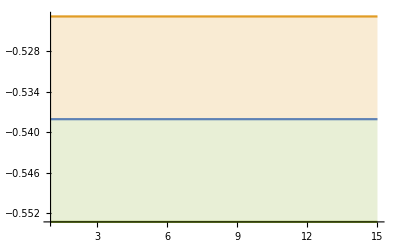

```mathematica
Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,15},Filling->{3->{1},2->{1}}]
```

```mathematica
SpoilHWFLOPlotN3=Show[Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,Length[meanErr2[[5]]]},Filling->{3->{1},2->{1}},PlotRange->{-1,0}],ListPlot[{Table[{τSteps[[1,i]],meanErr2[[1,i]]},{i,1,Length[meanErr2[[1]]]}],Table[{τSteps[[2,i]],meanErr2[[2,i]]},{i,1,Length[meanErr2[[2]]]}],Table[{τSteps[[3,i]],meanErr2[[3,i]]},{i,1,Length[meanErr2[[3]]]}],Table[{τSteps[[4,i]],meanErr2[[4,i]]},{i,1,Length[meanErr2[[4]]]}],Table[{τSteps[[5,i]],meanErr2[[5,i]]},{i,1,Length[meanErr2[[5]]]}]},PlotRange->{-.03,-0.005},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]],markerlist[[4]],markerlist[[5]]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]},PlotStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau_{\\text{steps}}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3(\\text{NNLO})",Magnification->1.2]]
```

-Graphics-

#### QCD LO - gauss

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={430,430,430,430,430};
NWalkers=200;
Nf4α1LoopBig={0.4,0.4,0.4,0.4,0.4};
aList={1,2,3,4,5};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
csvData=Table[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"],{xx,1,Length[aList]}]
```

({mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.06534546968841581, -0.06822597630146417, -0.06655104893802387, -0.07230164659640667, -0.07089699128749537, -0.08824969561673204, -0.08485990103414692, -0.09611475960381191, -0.06016539100078676, -0.07160803911436371, -0.07228692241641708, -0.0587233185845755, -0.07726287819472777, -0.071399108585499, -0.08445898330680747, -0.09965343497781197, -0.08866945768793792, -0.09215274047863639, -0.0703782850638996, -0.06464838894406774, -0.06966332051331658, -0.07925507355157023, -0.06606801989613602, -0.060442733998034646, -0.059123041172816714, -0.05078593932403806, -0.055280834150346736, -0.053733732260350976, -0.050800181568990854, -0.06248778872440743, -0.05261158034558932, -0.055614170083656725, -0.06194550263475215, -0.0635126902230833, -0.06468881054303836, -0.07020423174091714, -0.05608435512594474, -0.06492193572822554, -0.06295118724082567, -0.05719510515272825, -0.05501851386463538, -0.05587251565396993, -0.06165149176137646, -0.05854119019574486, -0.062159149565015906, -0.05561946977936409, -0.0610541323688921, -0.058888998126159844, -0.05821862049995411, -0.07437414820516278, -0.063912645019523, -0.07078409325092652, -0.06918879758875654, -0.06575049148413893, -0.06322362420297732, -0.06323775490368545, -0.06894786824096444, -0.10453277321255405, -0.07657338363581331, -0.09952969940156334, -0.07533328956172182, -0.06882622717088879, -0.06847474583951976, -0.06403724947431874, -0.06322970394482925, -0.06325957948367747, -0.06930210240748988, -0.06679459433025049, -0.05753080681532949, -0.08609622187029396, -0.07277967633004838, -0.07344689026499869, -0.07442253939943679, -0.0734039199217179, -0.07460423468207131, -0.0612255906870724, -0.05477753668324757, -0.05664434049633801, -0.056523085647986804, -0.05586875624777991, -0.05497741223925503, -0.057252472126893765, -0.061801947289600485, -0.06439294228545421, -0.06249632733133244, -0.062122752638057575, -0.07138579836674462, -0.06874578888220907, -0.07656019685798357, -0.07616054198896663, -0.07379110022098584, -0.07541717455439031, -0.06777551356973803, -0.06972797538042161, -0.06307437021873047, -0.05675884226553888, -0.05781627810243023, -0.06437085679814061, -0.07125285847485512, -0.06999039960268892, -0.06413224016875134, -0.06427491325154631, -0.06725388589378639, -0.06812386905722162, -0.0633792972783813, -0.06837411879987447, -0.06094036025464125, -0.06046822000098719, -0.05750401666615835, -0.05203676808720526, -0.05229409213657657, -0.060790319864708946, -0.0633481901136876, -0.059106952129358084, -0.06837697288665265, -0.06785577807764166, -0.0571100201454858, -0.0548912929189529, -0.05609792160425289, -0.06239417784893127, -0.074320640783514, -0.06527647693348128, -0.09435409828741952, -0.06534579826767509, -0.07304524186740487, -0.06215973597885785, -0.06394198760355978, -0.061583489899199546, -0.06021373361416751, -0.06682527845414865, -0.0820452984378473, -0.09016514939482706, -0.09191617209548016, -0.08336612952619175, -0.08714312428532588, -0.0890469636681984, -0.08939666352574688, -0.08614441075819702, -0.09015520636715606, -0.08291995672046301, -0.08628686661448948, -0.08420901546437987, -0.09281343497179946, -0.11938500085285576, -0.08875674536961406, -0.08363395611246836, -0.08942006837284641, -0.09237960973912085, -0.08983000028192353, -0.10591749012293107, -0.091345763400857, -0.0890428831719735, -0.09372020718553814, -0.1025651116569947, -0.10039886544102788, -0.10069382848412167, -0.09177121230713164, -0.09074553167107212, -0.08050521780178051, -0.08144121789035388, -0.08033310358184646, -0.08150355992177011, -0.08731862710131676, -0.0856436703431695, -0.07714674542710263, -0.0819347372367585, -0.07638938812932133, -0.08204998291330955, -0.0802235198004592, -0.08171164923971011, -0.0863545973606678, -0.10623492069106467, -0.08172763002225335, -0.08939195643029489, -0.0967812481915447, -0.0862922753363654, -0.07923247507831649, -0.07874591736186642, -0.07055081329852905, -0.07472629815764409, -0.0756054891179098, -0.07278520564470482, -0.07480300204413656, -0.06919477827317212, -0.07793239518374416, -0.07782742318527192, -0.07971339037358567, -0.08903721571852012, -0.0747052139533782, -0.08190630897624966, -0.06327607632757319, -0.08496103683233831, -0.058407341964015036, -0.06521009848033375, -0.052156717389932064, -0.05896017768929383, -0.05410567347172869, -0.05394129051281718, -0.06806189093663302, -0.060456460933907136, -0.06898627597353771, -0.051505754135305566, -0.046882826171999445, -0.046225929299858075, -0.047693340533071386, -0.04775558496127486, -0.04427221185185018, -0.03891483296913239, -0.03460020750384164, -0.03317987980927848, -0.03886937154040189, -0.05116318727430823, -0.05505513374965699, -0.06824133660041404, -0.05509367012684297, -0.07614305991036147, -0.05464140735054727, -0.06666448196606457, -0.0996215288453607, -0.10813020822134754, -0.06687557719184618, -0.05563728295994885, -0.05935984630860286, -0.0565501211210117, -0.055709558278400156, -0.05704650760953271, -0.058363277114301365, -0.05795236708982907, -0.057782398749543606, -0.05833590656460115, -0.06818030551223452, -0.05893042359222347, -0.05634279686632569, -0.05347250401342411, -0.06526649909691587, -0.07983192955237156, -0.0804722894652919, -0.06987606279639072, -0.06551659235217162, -0.07811042741222367, -0.07379872196466013, -0.0899457197241069, -0.07401820887984961, -0.09826378844257662, -0.08557809826150929, -0.07058625166238305, -0.06363178678550961, -0.06660996228652458, -0.08825174789358575, -0.07923194673710061, -0.10282812126495222, -0.1043267148367677, -0.8622455279592389, -0.11533259938816919, -0.10444521379704537, -0.07557322697256157, -0.08272239490591707, -0.06358125950048125, -0.0902295838669201, -0.0772878982143007, -0.07672044896840871, -0.08479688835220374, -0.07950133108426712, -0.06855762988523571, -0.06582905556920864, -0.06512757189350958, -0.0754214645702956, -0.08221083941610918, -0.08096670410005631, -0.07629291326086508, -0.08732176712337315, -0.0903232080248766, -0.08987861926379653, -0.08184299931887427, -0.08190626990972649, -0.08089109953850374, -0.06811619231780758, -0.06814870651655834, -0.09302192248366825, -0.0825541396176078, -0.08809836442479232, -0.08581110891972818, -0.059729906641970726, -0.06785321942777145, -0.07045533986646083, -0.06374581615551467, -0.06874711214244661, -0.0892436883749765, -0.12855516341994308, -0.09383871599894035, -0.08103335852801968, -0.07645916716221349, -0.06319753354681185, -0.08850675470731276, -0.07958439569275162, -0.11820253546414661, -0.10124099305817022, -0.10981832212274337, -0.1129520707444708, -0.10610404365355215, -0.1061853645133703, -0.10394495752593116, -0.09611965688321392, -0.10039677706768262, -0.09983942949754816, -0.08911538389522682, -0.08684312739015558, -0.08030599431189989, -0.09069510229963663, -0.08908539766785145, -0.07914899680380773, -0.09825156752594394, -0.09151143808822403, -0.07987157027824121, -0.07559462091937925, -0.08726616670727926, -0.12221164866663609, -0.10487931137876476, -0.08244942469223315, -0.08715891720704025, -0.06441316811298092, -0.06959825709352882, -0.07609490830083919, -0.07385514618602249, -0.05901964996522503, -0.07933841777457191, -0.08921916900808584, -0.09232983967857211, -0.07133021900223416, -0.07947118561890228, -0.08222304089992197, -0.08617277339261221, -0.08543960514670255, -0.0762582056384471, -0.0825473265218991, -0.07909054748543226, -0.08421300886040085, -0.10361085903818235, -0.09676612656890313, -0.07727280206331925, -0.03912345350839108, -0.03968627789431204, -0.043941443763200444, -0.03694752087284142, -0.047657040453605914, -0.05732902910369804, -0.04712235139613146, -0.03532231382548648, -0.03983541161630144, -0.04861137508440659, -0.05311915950429416, -0.04994621746708826, -0.05879295530356351, -0.0888566383566997, -0.12621827620256415, -0.11480263590303647, -0.09765390835713404, -0.09312070090310266, -0.09041221010642793, -0.10236693310634082, -0.08980480599761567, -0.08210745863751094, -0.09593070968739613, -0.0931567860720684, -0.09474215100661817, -0.08522513815473957, -0.10737074674792464, -0.1090858805090396, -0.09459880700903027, -0.09818858023415628, -0.09601608316561432, -0.09351384298059921, -0.08318612449336474, -0.07715825150897483, -0.08139334496179623, -0.1169640726046173, -0.11411439098525915, -0.11310181607661257, -0.1273060758231103, -0.14178931429296013, -0.13283937789186032, -0.12313481575911615, -0.11022761682450719, -0.11748485504019501, -0.10959913803320366, -0.1263371106187676, -0.11648098372229858],[0.005590209183789939, 0.007901541682551621, 0.006619160165087503, 0.012377215753685297, 0.010700062976630722, 0.02769422005375869, 0.01826282483770758, 0.034796011772049676, 0.00837383409877931, 0.012468292401118849, 0.014379355262861366, 0.006541235173532746, 0.011894986929094487, 0.007524102849881694, 0.010949319739198318, 0.014784078483899614, 0.013092981823781805, 0.014992328899148586, 0.008176108567845763, 0.006664543702038322, 0.007878275282481981, 0.014965992007876508, 0.00839948006296467, 0.007519511999392441, 0.006640170772690663, 0.0045419124059187365, 0.005840254556110572, 0.006031113725469853, 0.0060380435124276965, 0.008517968259830191, 0.004993280733277515, 0.0084928776520116, 0.008339928998004977, 0.00873508003606709, 0.01459151943769796, 0.01031567395450561, 0.0060477738885936615, 0.010518518814811504, 0.010129092252607472, 0.007749371933270609, 0.007686579814823011, 0.00811799221328213, 0.00837962001648566, 0.007937527704242138, 0.008006860824959928, 0.0067108915175470175, 0.007381007427626419, 0.00762221621153461, 0.007643193019227825, 0.009960845125276207, 0.008601337246879797, 0.010161854457416747, 0.00973432404875729, 0.008302536630217761, 0.00970009857442059, 0.009980300446023238, 0.013600051878696215, 0.04274734928186462, 0.013740775643400198, 0.026774633497983834, 0.0111403677816677, 0.009720709121640171, 0.008374940359122228, 0.010849436904732656, 0.009097519484074069, 0.008188246369980381, 0.012718534683768443, 0.01217858925689439, 0.008890431882804717, 0.018389108883481716, 0.012159530831195371, 0.01011238385232692, 0.01274424366042853, 0.011256521604651386, 0.011064205691464912, 0.00857091290687944, 0.007236864814672926, 0.008503735687356292, 0.007622514454999702, 0.007449265681834201, 0.008191645689160445, 0.008511431022466385, 0.009373298311272198, 0.01180675690784472, 0.010363821426142701, 0.011695897869085203, 0.012728985228122497, 0.010349782227141058, 0.012535075988727887, 0.010501767361332572, 0.013289596872411172, 0.011546586474895608, 0.010604596131502364, 0.009987174250934231, 0.009330456761986575, 0.007688561295836133, 0.006597777906771171, 0.009906976704321587, 0.010128172362826525, 0.00913411519821316, 0.00919743528893885, 0.009680782743942386, 0.0100391754484809, 0.01157272828416269, 0.007943364654071337, 0.01072054762788864, 0.008461344684960992, 0.007022587242212631, 0.005800421905213557, 0.00507920914487844, 0.005686337875102088, 0.007675968106103287, 0.0066536256087483025, 0.006049831933766382, 0.009840952183273842, 0.01155950956456465, 0.007477209052328338, 0.005625963937998207, 0.0061918152494397334, 0.007276424459090505, 0.01018987256180597, 0.008674617352434836, 0.026945100936322047, 0.008979892649520508, 0.014632679686224769, 0.00825160048116201, 0.008284405582693274, 0.009217674956510663, 0.008851233769921907, 0.01161695291772442, 0.023036031366706414, 0.027634928986227474, 0.029730572282645584, 0.027980295883661695, 0.0286450199725152, 0.025928953538054137, 0.024986467341698116, 0.022931688538674208, 0.02829752621818959, 0.025433418856148044, 0.024144542936523003, 0.019150345418331174, 0.019973960453077554, 0.03140747959481992, 0.021191015003043438, 0.01994148032589173, 0.025723619688015467, 0.022340719146092158, 0.022600511341850545, 0.022583773581149685, 0.017505885408870957, 0.018281721814846504, 0.021263944554640812, 0.024706634738976857, 0.0259573428240893, 0.02412887618628503, 0.026980807747889454, 0.026636328917944162, 0.02374951272261357, 0.023127398060005386, 0.02268675932342071, 0.02263173635379379, 0.02307748069586016, 0.021511780451534526, 0.01870751220708563, 0.017680174151794285, 0.016337218953655395, 0.017008969026389216, 0.017796291821099305, 0.017691312198901576, 0.02039403877272663, 0.033001192376126955, 0.024332314855009602, 0.02625864381127087, 0.027506282140371863, 0.024915011852647904, 0.025007834662171696, 0.02359358707513398, 0.024866219397561923, 0.023502000333287757, 0.02172902507371959, 0.019971493583951935, 0.017627538290105917, 0.01687835296276855, 0.016939075581124854, 0.0186212102827443, 0.01791111540053039, 0.020893417458562016, 0.017800670900278436, 0.0270600298226383, 0.014719244625777554, 0.029220220953065174, 0.013223604054467592, 0.01221802003666791, 0.011601309351860468, 0.01447925899020833, 0.010002494339014699, 0.007746705702908882, 0.0159077913667755, 0.01141359569236449, 0.02213456954886512, 0.009963139107647926, 0.007789007449202741, 0.0070865207685242935, 0.006671295365358663, 0.006901234595962894, 0.006366168632231148, 0.006247929016667489, 0.004719026368615164, 0.00559987713169442, 0.005353403953418504, 0.010199678258529125, 0.009997748675278056, 0.019063869600342412, 0.013991475571986626, 0.018984981716256427, 0.01169190949102371, 0.013247092064347024, 0.035447777743281984, 0.04492326931441556, 0.0126560008180126, 0.008426057186388846, 0.01241377096050851, 0.013242448812610465, 0.011806372762299053, 0.011937037334593573, 0.00991356060615938, 0.01043633844883316, 0.009962413338536842, 0.009274662286217364, 0.014724433744506956, 0.008928407931641562, 0.008265107654605941, 0.010895926472385067, 0.0151053627884326, 0.015849584775274574, 0.017688007961404652, 0.01580031382641166, 0.013797931474883236, 0.014813427988314844, 0.013655646819714614, 0.017859242433197666, 0.009960203911768122, 0.03226992513647128, 0.015379222701499903, 0.01301039137271125, 0.010419244417222837, 0.011020930382294385, 0.017272134443219855, 0.014154151367777399, 0.018346559524339945, 0.021209361171472017, 0.6394395643459746, 0.02330519004875233, 0.029177713359346897, 0.01695021800318106, 0.013636675451185881, 0.015972016623606283, 0.014926004780473038, 0.015614168696648481, 0.021929040378382204, 0.017748653591434772, 0.018317593679414924, 0.019516386626081305, 0.01794841892921564, 0.01917308751905116, 0.01806701559599604, 0.019664678426326836, 0.023564911347500227, 0.022127169430190236, 0.026780413491045065, 0.024339518652321892, 0.024979676876454953, 0.023164286775826267, 0.026168709883433245, 0.024746526672517536, 0.019725045192693382, 0.02010744868768335, 0.028120674355144776, 0.023799730848981255, 0.023649773350426957, 0.023576356320858055, 0.015356563504663788, 0.01971048897844079, 0.015935071188206435, 0.009690909124320924, 0.013899948593596664, 0.018509026977293737, 0.04335186334428618, 0.015327144342110327, 0.011389107515356463, 0.011570475236566504, 0.011298578541452251, 0.025488621247427814, 0.022271608860121386, 0.03510667932979645, 0.03618998452744096, 0.050294677858561725, 0.05110211884515744, 0.04713473737058676, 0.04731409887467847, 0.041981492699268465, 0.0435790084614425, 0.048758032450132556, 0.04069273096027938, 0.02931716504112676, 0.018514128673147535, 0.019716182786974002, 0.02474435006893352, 0.02354597588118625, 0.01562600321313829, 0.027425895507058137, 0.026448342714729667, 0.024211380391854512, 0.02328454158011493, 0.030345117112413184, 0.044774358741914384, 0.03523844855675745, 0.0207308463262343, 0.020044320600805375, 0.015316885430371482, 0.01698730390594299, 0.024027981012626185, 0.03247714712681538, 0.024477943467062016, 0.0190680308480345, 0.014643259655315662, 0.018482914015227444, 0.012302538530166296, 0.013356989888922827, 0.014805264195911274, 0.017430680579655564, 0.02025988277926558, 0.014151481691895274, 0.015614418858353527, 0.014910617689692129, 0.023590068722791374, 0.033630515654480934, 0.02781536955662226, 0.017837162521785806, 0.008383382982909103, 0.00540416201993391, 0.005294450881999326, 0.008963407801871772, 0.009940669261266896, 0.01060808315170308, 0.007482076502614712, 0.011210403851285022, 0.01305349271653566, 0.006705817103875751, 0.007018046334647857, 0.008956716634628886, 0.00852576865863668, 0.01859209251689486, 0.03660706174816902, 0.03649946976899787, 0.03150337053744476, 0.026232391781057296, 0.026270740209254958, 0.03500887663618457, 0.025251621874584587, 0.020582979269902366, 0.021690030023992567, 0.02230780408028714, 0.025992120815392813, 0.015440208324339464, 0.017156236426783322, 0.023367670606311113, 0.02049118212846159, 0.029043942974840063, 0.028994587172670564, 0.028940297028502066, 0.023010786420188004, 0.012755059363749427, 0.018808895470642625, 0.04293730872809389, 0.034579803746834004, 0.036446864202746336, 0.04873505229214607, 0.05383871365082339, 0.04818884558833068, 0.04207885835667721, 0.04527065747718355, 0.050538713880294774, 0.03717669329783381, 0.04993416761385044, 0.03839308383044086],-0.0584901,0.000805775,0.728948}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.057862543585027564, -0.05842356570804846, -0.06647213320967887, -0.058296260755410056, -0.05878660606347497, -0.055992868665778114, -0.05715505547825222, -0.056380460495222114, -0.05917601224498749, -0.0620637674949999, -0.09124996406355969, -0.07085413600973993, -0.07005024135460508, -0.06814129792861807, -0.07097075027720559, -0.10793613082791603, -0.07669534212202483, -0.06739675075279052, -0.0636701254048812, -0.06961223983911546, -0.08098867752653445, -0.0734891758104986, -0.07805850776357585, -0.09167931513777532, -0.0748147719555777, -0.06724000078767782, -0.06519947321976464, -0.07386846071148487, -0.07295363666294882, -0.06781326946397373, -0.06494436489716499, -0.05956523537135809, -0.0592759660176811, -0.06397066294099386, -0.06358317673565805, -0.07779252061085777, -0.08282574014832925, -0.06708314271383918, -0.06772922017705568, -0.07267227887599044, -0.06536283256169513, -0.06657258725537303, -0.07340420381084498, -0.06546948120794671, -0.06362024350580804, -0.06503417345581873, -0.06829435976559126, -0.0709088670371961, -0.07210154501262028, -0.06607139003323945, -0.06562791965240361, -0.07485779010254774, -0.07524686204855319, -0.076579294129414, -0.0665192523269174, -0.06455525184471618, -0.06892958753532052, -0.07199694264991895, -0.07623617454740354, -0.07452612607384294, -0.07160496372366455, -0.07540287592328747, -0.0683253455081531, -0.07109611100875038, -0.07386485879838552, -0.07112721180985003, -0.07478748993893782, -0.06942765039123003, -0.06786400207169466, -0.06925602353845949, -0.07380869153590068, -0.07900466526595806, -0.08068547451446105, -0.08712061771939346, -0.0947879139114008, -0.07180961052378478, -0.0672006293352906, -0.06629532205879565, -0.06771446029703272, -0.06867584972115444, -0.06983152518561521, -0.06623766332827509, -0.06303721339077545, -0.06676119844056252, -0.07214953812678052, -0.07525194764052479, -0.07306904824374101, -0.0786741189123177, -0.07997353338333504, -0.07915127703826252, -0.0856829729446566, -0.12409289318263528, -0.09594170717506934, -0.09478282016694067, -0.07747004801102281, -0.08242007695015222, -0.2118573577631755, -0.17170705644788428, -0.11738455106948661, -0.27061301866298415, -0.12841835714954908, -0.15683700646670948, -0.21604026714408264, -0.21355468751938553, -0.25249519656719177, -0.23542405781247605, -0.10770742131152337, -0.10845623796694212, -0.10031216008703411, -0.1139605814568002, -0.09675541882373917, -0.08356777622221132, -0.0819078155668315, -0.08151217655535792, -0.07867437535747566, -0.08011858245927606, -0.09025390105238333, -0.1344219609059437, -0.10436425962412528, -0.12083207821582569, -0.10363176761842355, -0.093059301544049, -0.09645051776961902, -0.09524686317159724, -0.08387510457450915, -0.09210810276948536, -0.08575235528201282, -0.08383449518909919, -0.09481174129213553, -0.08972745715524016, -0.08237875573081441, -0.07131159474039755, -0.06888023916053321, -0.06382040773227678, -0.06989588289382034, -0.06874978661273719, -0.06365359528776666, -0.06184772770660783, -0.054923913353879375, -0.05517567035912763, -0.05796624500110824, -0.05652658939751006, -0.059495478633425435, -0.07670505767104803, -0.06190726172855984, -0.05654766406760604, -0.05506760578514096, -0.050419371492550234, -0.051395724296986, -0.05411501405254169, -0.05172327367494637, -0.04793812152346628, -0.048040599585009565, -0.04873205636010138, -0.04697744108963247, -0.04502947565373307, -0.045628378773186117, -0.04629351222544798, -0.0460938890391351, -0.04606419858299443, -0.04671813250801267, -0.047316605242861874, -0.04645976219976838, -0.04713732222884491, -0.05054929151926921, -0.04982285560783457, -0.05436623431376516, -0.05413191559279785, -0.06360356451704184, -0.06298470288365533, -0.05454157643694078, -0.05182004395686923, -0.04924693837157654, -0.04836205757128934, -0.056552583006698215, -0.05062267440589992, -0.04793717434818616, -0.05048138838568117, -0.05356230741136047, -0.05430751898183873, -0.05274150455387006, -0.04981777123257153, -0.05074133214419345, -0.04905888600638374, -0.04898462171859454, -0.0473033269893261, -0.0463950259762665, -0.049559152749679036, -0.05171362845122466, -0.0644282205458336, -0.055060754196618426, -0.054931585105585705, -0.05366628422856722, -0.055505124817021044, -0.060780161473697476, -0.0658774750108567, -0.06687336381385565, -0.07128932966792637, -0.06399761431591292, -0.06723338060615366, -0.0692626727569153, -0.07479184570650554, -0.062364376332957466, -0.06514602239643114, -0.06764420830505755, -0.06654010476412871, -0.07226886332373979, -0.07441653612391728, -0.07455742208563129, -0.08552068605121123, -0.07187533614805454, -0.07590724623467845, -0.07633522022694168, -0.08574733477990862, -0.0838859615123568, -0.07141328757285467, -0.06346992370036138, -0.06668525729500062, -0.0582691849049811, -0.0637763815492285, -0.06468283604936115, -0.06080181380796198, -0.06380220790126558, -0.05866067042254649, -0.059320954485323416, -0.06030177954430016, -0.06341377575964526, -0.05380540271316269, -0.05395864011754538, -0.055209968956568975, -0.05167505704009344, -0.05338603022056332, -0.056757775951579756, -0.05389653507335025, -0.049703220408735135, -0.05229804813292913, -0.055359626400476175, -0.05917629404480863, -0.05742460671114697, -0.05582127478305948, -0.0550948621679029, -0.056287038250669386, -0.05867345966606464, -0.05872381540882007, -0.059421180523225724, -0.060175914964031206, -0.06429700915414341, -0.06167174152897399, -0.0643190576966275, -0.06942245205774362, -0.0593670829047267, -0.06352362330236845, -0.06316451481722872, -0.06047166670289376, -0.0584940420640342, -0.058137395287379726, -0.060600194991893, -0.0640321001238973, -0.06386501735607689, -0.05672485151871387, -0.05705083751587776, -0.05445260033899404, -0.05483750395799394, -0.05538632374502314, -0.05175121429700514, -0.050693561097418, -0.04927035806794769, -0.05002871774332755, -0.050336046011766604, -0.053898905505823276, -0.05512229397681982, -0.05521695810227192, -0.052610222015077465, -0.05314474943181315, -0.05298398482622907, -0.05519179810434259, -0.051989282708188936, -0.05371579528367451, -0.05335590004969432, -0.052811747756319374, -0.0528776209632486, -0.054049706015175995, -0.05149091238236169, -0.05098062785757592, -0.05116886506383186, -0.05307240301956403, -0.05169988789197326, -0.05181687097656878, -0.054339793630675065, -0.05594578484160668, -0.05595274026123401, -0.061856041289272364, -0.07666436512428829, -0.07109385294655661, -0.07457012404871129, -0.0677880624046935, -0.06733298528423382, -0.06873030917493353, -0.07524192024465741, -0.07360962573226248, -0.07644018149587418, -0.07763723708377189, -0.08870700596563699, -0.08306816858096609, -0.08216667642725001, -0.07836483360560133, -0.0724806353221231, -0.07512170867035142, -0.07363267567526571, -0.07538801938817564, -0.07702149813877415, -0.08107740208740451, -0.09131364631780424, -0.08455539640140591, -0.09662726280649767, -0.12312659396003353, -0.12090707118143859, -0.13010413568925794, -0.13954624208001945, -0.14057909857815315, -0.18858983374385285, -0.19489038779101303, -0.17031314363637554, -0.16904489308318638, -0.13394735333644742, -0.08945512085014894, -0.11438039670790047, -0.08477365341142061, -0.1044554615842104, -0.17349865985839938, -0.5999990343038828, -0.16731776261601133, -0.24233901760673118, -0.1943628107965236, -0.18464267713921229, -0.40783957510995, -0.5220097232685811, -0.15272499380224244, -0.13194542157124248, -0.12675657163416656, -0.13263337878460763, -0.11746155240879441, -0.1300706731733492, -0.13062313211919163, -0.09674870642800823, -0.07818719818762844, -0.07336309095925238, -0.07433513362608957, -0.06813991181112947, -0.059392276676521985, -0.058984743609650794, -0.0543704852022533, -0.053436192559732636, -0.052957198301484536, -0.05111266935719712, -0.04548674712331019, -0.05180244360575524, -0.04923678782560822, -0.054814863705870374, -0.06739138139713803, -0.09300556431859146, -0.10721977547363491, -0.10454301377978492, -0.09150594175343266, -0.07291849804783111, -0.06367212651173111, -0.05458520782949282, -0.0575521257691006, -0.04998437108943677, -0.04545084589396006, -0.04266537217390028, -0.048398720308560406, -0.05159031776753527, -0.04991744838637582, -0.06021597536342901, -0.06675021351303334, -0.07093074426094682, -0.07265107595674009, -0.05541171783563223, -0.07005004543879007, -0.07531055095235818, -0.05907990327106787, -0.06288596583532526, -0.05636426109740173, -0.054259103903783856, -0.06327317791502153, -0.052742586757700015],[0.0038534196760018256, 0.004043730737976108, 0.008980164664870468, 0.004221170843052708, 0.004426806937840994, 0.0036684750950949853, 0.0038831157584733184, 0.003773757674326501, 0.0047981924481776, 0.006738407767723137, 0.028340425422142927, 0.012244679841665638, 0.00958152757332751, 0.008448826858268687, 0.009208769113340762, 0.03639352716390056, 0.012591275794587799, 0.008084776182043518, 0.006107563957648115, 0.009418978179278635, 0.016904960384699082, 0.013025213420429362, 0.013841030200987767, 0.0213149153620601, 0.012262074881030805, 0.0074328588234472475, 0.006135024697593443, 0.010452775525935426, 0.009945275748895449, 0.008465102944034315, 0.007760935378602369, 0.004814480845289906, 0.005296427699831602, 0.007447870613694391, 0.009153603412793742, 0.017784730324568607, 0.01878649406440027, 0.011197228537887566, 0.009286838845544007, 0.017043799131865073, 0.008353995876957392, 0.009601796605443622, 0.018618267335369407, 0.013675862466754351, 0.011802446571473476, 0.013250114987017897, 0.015723965142737346, 0.018465485403409376, 0.018254941586717418, 0.011533139274526451, 0.008528061582092926, 0.015447766873530817, 0.013146977201691447, 0.011142692862878356, 0.007133512950082767, 0.0045410993650490195, 0.006201746640027978, 0.008055988149638363, 0.011202046118818821, 0.007180631734100365, 0.006197132007736985, 0.007300278466021597, 0.005459522196506663, 0.007380509378265101, 0.009917059898617757, 0.006756083868490628, 0.012042577843545987, 0.0061629028126931025, 0.00836563756138051, 0.00840701083911848, 0.011619922785011262, 0.014992942251572591, 0.013462359211369524, 0.015658205463637425, 0.02077143019199931, 0.009652462580591513, 0.007158187935781837, 0.006154056610627225, 0.008615271257942234, 0.009527395993270165, 0.009585136038902311, 0.006359328738531964, 0.005802794539651381, 0.007289145176152119, 0.010511794211922337, 0.012855581564681319, 0.010583341108967735, 0.014440049296375853, 0.017291956698013016, 0.016091097982078733, 0.02104465474425718, 0.05307191663376326, 0.02325500918851442, 0.03046171872581918, 0.015544715365938244, 0.020400534674247524, 0.14036880115876962, 0.09843055495325596, 0.04947875412105945, 0.1758738483540538, 0.05861949220890646, 0.07912533968122752, 0.1234295540334392, 0.11410045423938797, 0.14337347176831913, 0.11861969240207801, 0.03475216156260951, 0.03270593967636094, 0.02237446030613738, 0.03188248928927569, 0.018203630570696034, 0.012254155026204068, 0.01176620638809653, 0.01183343185620401, 0.009604639893498931, 0.00994666319439925, 0.015315397271111881, 0.042264613266431154, 0.026241678074617247, 0.03720781954630008, 0.025553312345002063, 0.014875872636319575, 0.020022947493064033, 0.01645512402961433, 0.011643071539602515, 0.015115220376708816, 0.012061020563751492, 0.01171656829374723, 0.02432644917877062, 0.013161866008123482, 0.011768926272832799, 0.007961372150380648, 0.006075008299812591, 0.006388016520477602, 0.007040889373569807, 0.012138291484021351, 0.008895387415525001, 0.006516987963377271, 0.0063870904591998325, 0.008574317247996822, 0.013063296128793426, 0.012416119942127895, 0.014470070606614066, 0.0340358130814095, 0.012183284556318084, 0.006112354462404891, 0.005226613723358603, 0.004852942383498753, 0.006669557326702822, 0.009673260790491715, 0.008624791013039623, 0.006266218857325196, 0.005569220552270266, 0.005019872500232616, 0.00524576805932797, 0.004429778629268001, 0.005258118130284552, 0.006461170116916937, 0.006025761094438222, 0.006167792986178912, 0.006006457782376863, 0.005273529165399141, 0.005272808300541072, 0.005210330689244986, 0.009290011193443144, 0.009152363996512597, 0.012879098692231057, 0.011682580567016444, 0.0228505905407828, 0.019400248901346905, 0.009652801033861897, 0.008676840508027969, 0.0071102634584238236, 0.006474105306487028, 0.014243031792013075, 0.007982513643144536, 0.00617511165191373, 0.007219701646364073, 0.008114390075888071, 0.009206363028272513, 0.00772416679062197, 0.0068219093199895975, 0.006711485811160739, 0.00591020261859572, 0.005896691834078138, 0.0068268175660796005, 0.0059722449524604, 0.008983458119674655, 0.009821357477113329, 0.019131175537376116, 0.011723113799227011, 0.011048841698400147, 0.011565291886215722, 0.010553765716140008, 0.013337597996772466, 0.01777082855356837, 0.016924304012287568, 0.023296516052936058, 0.016904935544529938, 0.01988840808385654, 0.020099548854188676, 0.021563480215657852, 0.012642136762878875, 0.013800052967097146, 0.015087185384052276, 0.013231324647348764, 0.01385704305737097, 0.016940190453405585, 0.015311060575567624, 0.021077033571768846, 0.013939692861838283, 0.016165853497782604, 0.016783655342653896, 0.02584882279368431, 0.026051665255493784, 0.01733399643556625, 0.010107302747502928, 0.011073297006947834, 0.00823421459966868, 0.0123986649211952, 0.011742518671746789, 0.009587208364742054, 0.010760765192066597, 0.00710486401171059, 0.008112815991226692, 0.009067893520599097, 0.010617753526527218, 0.006072395899252987, 0.00586141299423737, 0.006339118838380238, 0.0051862895880329845, 0.006119741339177332, 0.007999454101175883, 0.006162645049946491, 0.004960485694480992, 0.005592243200486134, 0.007855807854304817, 0.010071957122255878, 0.009072996179691243, 0.007707929229825944, 0.005957157029378618, 0.006277708012363971, 0.006368606094677397, 0.005553240894077946, 0.006945847149443455, 0.007658455745845877, 0.011194254664681855, 0.008538390785095818, 0.011137807176754078, 0.014208083388805894, 0.008091459843207117, 0.007042637873710956, 0.0076400472832541585, 0.007143206738589436, 0.006425672639923392, 0.006769264298443363, 0.007908721152129553, 0.010856677419426615, 0.011853528760485694, 0.00736692478518895, 0.007531002017810014, 0.00608797416654938, 0.00542716764077331, 0.0045657411853131736, 0.004060023049414327, 0.0038433535564565847, 0.0036575105427893405, 0.003716235238766253, 0.004709936284252086, 0.005272992791019262, 0.004406573881287999, 0.006174326098998343, 0.00701980040254137, 0.0067753657836524366, 0.006495821236449831, 0.0079318088694949, 0.005589974418018122, 0.006202700675159543, 0.0059405338005955955, 0.006006762625547769, 0.006271350131278891, 0.00714581600571928, 0.006360564521923994, 0.005158986665530884, 0.005259658520155384, 0.006423960627122307, 0.004437284028691963, 0.003671000617071369, 0.00608674779011057, 0.007418222191466922, 0.007662874539129024, 0.010450231428805808, 0.020535424576906283, 0.014169610588644061, 0.016201217126165103, 0.010403916884560507, 0.008268769954089216, 0.007341515534124177, 0.008706264091939158, 0.008341401650971367, 0.008675050594168116, 0.008466132907959658, 0.015498893328921069, 0.014527174123389061, 0.0161136590872499, 0.011833628978668824, 0.008556417560461252, 0.008320619869665022, 0.008102972161888223, 0.010311789913500196, 0.008557983353989856, 0.010151714628554562, 0.013879119374443813, 0.010812019629208728, 0.014915243365136267, 0.03454259358200012, 0.031431908466983245, 0.027049283208838235, 0.04272396233808292, 0.03786234430686048, 0.06915888858445195, 0.08901732657332906, 0.07371695068910965, 0.07593894089385346, 0.05349255551867653, 0.0220432118390282, 0.04380033518636043, 0.022457340142819984, 0.037083160472072704, 0.08709996067044162, 0.39033307027077896, 0.07985732941379207, 0.13042053794190012, 0.09474092455741753, 0.08735619417478273, 0.2298739287372983, 0.2918704837295109, 0.060594338780734565, 0.047895601156503056, 0.043978659558832865, 0.04682074437113101, 0.034517637875284994, 0.0386671240326215, 0.037105316373701895, 0.020328092923989655, 0.02199473113418009, 0.013968715954534052, 0.01640142914120548, 0.009583425997583666, 0.008359079228155762, 0.004309863562354713, 0.0059513987357769395, 0.004025810826081504, 0.004209847778666562, 0.007009734924040496, 0.005178707061933135, 0.0028331246396347052, 0.0025867682960408482, 0.003208416936262095, 0.011529429520733691, 0.026552959667500722, 0.03457353483052322, 0.03199561980953986, 0.02494474286942673, 0.014336487157329278, 0.007802739199314864, 0.0034250289628735965, 0.005955173555056912, 0.0026116833706533206, 0.0019084865990523078, 0.0034942177395857984, 0.003510173566110172, 0.003939036537431428, 0.006398113954575409, 0.011556598631410652, 0.02994782527671853, 0.022520147566099342, 0.02856319410983974, 0.011903940002648735, 0.02720102227767384, 0.020032553066110598, 0.010015758801600003, 0.014194144276205418, 0.005574616321261721, 0.004343765397078632, 0.008214703076332841, 0.003578147479867623],-0.0539854,0.000497897,0.638707}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.042713035007991396, -0.04395112833447303, -0.0424782865908267, -0.045373230350734144, -0.04354690206798392, -0.0425299963193773, -0.042638003456634155, -0.04241226686334406, -0.04135678664161452, -0.04143411494984054, -0.041306520987070765, -0.04152839586145172, -0.042342872202189234, -0.04167866639724751, -0.0412299938500107, -0.04127018322285724, -0.04150597088670613, -0.042458200952436916, -0.04282600220013574, -0.04405340803967126, -0.04562887480907781, -0.04260773267796566, -0.04204671023656141, -0.04308385995639796, -0.04386658016024238, -0.046798580445716, -0.04611593543195336, -0.045234562674926204, -0.05121396578535402, -0.05531353081728216, -0.04749032135110572, -0.05004301027259469, -0.04943149669865413, -0.04800772831049204, -0.04573812890087395, -0.04558452776789507, -0.044791622225654054, -0.045444239616451707, -0.047453558952407576, -0.04855997149450897, -0.04882473115942396, -0.05073467797099421, -0.04955042201973596, -0.052660381891249865, -0.051855798415736454, -0.05168843965698594, -0.05199396305661502, -0.0497239515263859, -0.049490911460838075, -0.04771862962559408, -0.04724734498308107, -0.047016311969500416, -0.04603173698364346, -0.04927756217222806, -0.05615169460462111, -0.04823970912803771, -0.049700216788418745, -0.047937407725313956, -0.04730549377750357, -0.049551880146237584, -0.049312166472970376, -0.04943688294753804, -0.04716962957712012, -0.04828724803254739, -0.0500638281184814, -0.05008008230185447, -0.04845582630977729, -0.04852882999658965, -0.04666360548747471, -0.04537218327473538, -0.04713821340692721, -0.046307799625497734, -0.047142193957521956, -0.048284335718415984, -0.04568581550696755, -0.047610737593715806, -0.046748311773974045, -0.0479340152156052, -0.046798188344347326, -0.04702778563399916, -0.04993037405869363, -0.05032627874846575, -0.05139471319278239, -0.056862341112830124, -0.05084966582836517, -0.0559552865590277, -0.06696876815963891, -0.05542579578204432, -0.05482101296508334, -0.057179780309872086, -0.05789256359222927, -0.0513023632310748, -0.050279308961558, -0.05067779320419229, -0.050159488069392216, -0.05241650478132204, -0.052660175986226486, -0.052709901392095936, -0.05208145289534581, -0.05267466531577036, -0.050587735687399264, -0.04985453557835701, -0.051690623093658086, -0.050667890050417635, -0.04910329371236857, -0.04985666040462532, -0.04909139298119772, -0.0493179592099885, -0.050129854178269984, -0.051420758024359026, -0.054130022793926785, -0.05737590598957672, -0.059473441895684834, -0.05669876574347539, -0.055348722696613305, -0.053608447835805595, -0.05624177438609722, -0.053487403041832776, -0.061136230060409955, -0.0742957329549387, -0.06796233475618194, -0.06374602374192269, -0.060287994467596306, -0.05796791128615666, -0.06421910533100857, -0.08942646449549072, -0.07894959068950731, -0.0795101178032679, -0.06695313322047117, -0.06606330212614649, -0.06575455807944275, -0.06226714093829585, -0.06308549483844272, -0.08110223286614548, -0.06558803631925697, -0.06239845552056973, -0.06453514895363911, -0.05988509225215896, -0.06103357187728567, -0.05821331519396761, -0.056216424414085676, -0.05827623418859171, -0.058243445599518974, -0.05764643952085998, -0.0588364714794104, -0.05796955288150344, -0.05656695325025453, -0.05517693304012239, -0.0556249636854121, -0.057367692599785795, -0.06560695181647382, -0.05597186912724615, -0.054809690208306734, -0.05501788963704719, -0.05645419039500953, -0.05875149981625341, -0.06074386880780079, -0.058270891544847325, -0.05617425226612119, -0.05491927066036626, -0.055860862776634775, -0.052901213846379504, -0.054977188820652084, -0.05701137433126875, -0.05698527240819443, -0.059037796804843945, -0.05563633264291553, -0.05179987940213425, -0.052076858192153706, -0.049127579684986884, -0.05029088676545319, -0.050257492048591375, -0.04989987894692565, -0.04938634125766616, -0.04890601275431962, -0.04716223879534578, -0.04819137669536827, -0.04710456193872753, -0.04690260720694979, -0.046914598571124115, -0.046303538790381744, -0.04620795312635249, -0.04825386961933383, -0.04688484977604592, -0.04815826268925406, -0.04941296627657056, -0.04920435888921109, -0.050192934419178624, -0.049844263047681955, -0.05021906780288564, -0.04992091850022332, -0.04998867842709546, -0.04983631323786232, -0.05383176138609482, -0.0549952129419652, -0.05658917607510028, -0.05291843359887841, -0.049096993359244084, -0.047025944118096165, -0.047471782694895215, -0.04883913166879802, -0.0477716898512005, -0.05584191370639917, -0.050418794656605544, -0.0518273216710013, -0.06001526516761475, -0.0563620523428669, -0.05751602191796243, -0.0701433375061265, -0.07450887545822128, -0.0785940095221847, -0.07601537408447953, -0.07483416543573039, -0.09251271488137348, -0.07081461682706347, -0.07570669448013566, -0.060446036086055865, -0.057725168492475346, -0.05820436083135298, -0.0574759290912839, -0.05593792978382198, -0.06325134741419498, -0.07843727692165159, -0.1537077539004152, -0.09806486940498473, -0.08110958967991524, -0.06903665919604877, -0.0635526503205436, -0.07039848552354226, -0.06814261603334008, -0.062380170763460766, -0.0606979603939694, -0.056707688731629714, -0.05840751956970144, -0.05504907160361075, -0.05552743148143935, -0.05621987177518566, -0.05479425132577542, -0.063045074110418, -0.0617124817115498, -0.05825330682859029, -0.0525398807173063, -0.05450131086767409, -0.05709578490455696, -0.0568324760800407, -0.05417097180380852, -0.053640342560477464, -0.05315750010209861, -0.049837315446524984, -0.049744458665447425, -0.04922361787467212, -0.04990041137925837, -0.050698543943030396, -0.04942809097564509, -0.05172624475632207, -0.054949139112571356, -0.054175382810558025, -0.0522274260678327, -0.06371719912894065, -0.06483225197162806, -0.07144344876281536, -0.07258780017070329, -0.07004896829285663, -0.06883756943321058, -0.0685019901653208, -0.07132563694674818, -0.07545411479820634, -0.06951272216103585, -0.07618269025886205, -0.07348450602432695, -0.07311002121240517, -0.0777554518813608, -0.07638214823328929, -0.2841048149775906, -0.09583952891526068, -0.10492602790572085, -0.0735609910915867, -0.07053917256029434, -0.06928885970716163, -0.05830135398348598, -0.05825633236799987, -0.061025042599856597, -0.06184372892264376, -0.06081135226937331, -0.06827747793594459, -0.06208866306500793, -0.07388570168719992, -0.07140021413789273, -0.06756617135913225, -0.06952308381329964, -0.0784867829897174, -0.07914126322836774, -0.07115922126196328, -0.07841741406470154, -0.06603374977194237, -0.07350394083847905, -0.0869775733948527, -0.10427207900886008, -0.08879147103459503, -0.11144089341794666, -0.09939137410460659, -0.08396342240534298, -0.07890907184844945, -0.07643675667913419, -0.07200741992061263, -0.07198985906197819, -0.07251088910533422, -0.0779962247225019, -0.07501075224851192, -0.0767644945655751, -0.07579127394192268, -0.07219273580329083, -0.07157915027007439, -0.07204165949410124, -0.07611944481468653, -0.07127560516516403, -0.08593388392510878, -0.07226328517381322, -0.0690441991597686, -0.06954646297076965, -0.06881026963695057, -0.06449924841688853, -0.059341333744737046, -0.06270615357829606, -0.06518174206232098, -0.06594994496659452, -0.06481261747671879, -0.06579641385876367, -0.06595213489473564, -0.06200235503127879, -0.06042020188990359, -0.05833825771727508, -0.0585009706468925, -0.056160067101067336, -0.05183627131844423, -0.05233246888835266, -0.05201755379512731, -0.050774969831054825, -0.05052448084283067, -0.051540967574564875, -0.05162650924670834, -0.048697549071531086, -0.04874094010104098, -0.048463897083637686, -0.049516116735878704, -0.049949151886791054, -0.04861727718296886, -0.04782573126324064, -0.0466838481345797, -0.04522833951091241, -0.04352009672324691, -0.04316531640844534, -0.04017755969432258, -0.039312904748769986, -0.03954978916631257, -0.03827025838392229, -0.037666648227735064, -0.03729594365557637, -0.03808705149693928, -0.03833312292293877, -0.03864953007507133, -0.03936447302994339, -0.03918594911258305, -0.03900582494045066, -0.03776717791440801, -0.03775229782415208, -0.037119320505037696, -0.03721575914642344, -0.03753181808771157, -0.037019157055787344, -0.037521437695220206, -0.037647470900567706, -0.038612228225480966, -0.03864337220885046, -0.038802367264452756, -0.037873447881098914, -0.03859149053643543, -0.0384304752739092, -0.03764467954865293, -0.03806508195660428, -0.03801240951367636, -0.03817753153927262, -0.037780480659455815, -0.03729804623688938, -0.03908638117227107, -0.03925526431993818, -0.04037226303095933],[0.002291814908712625, 0.0028823287051820837, 0.002182268408239744, 0.0038055230388800098, 0.0023971344208507557, 0.002169689985408017, 0.0024098949316026853, 0.0022282129514364637, 0.0018136709142993494, 0.0018853376892810643, 0.0019121024050233132, 0.001905006636022428, 0.0022383541910005684, 0.0022924590746959306, 0.001997736448196553, 0.0022174896741717193, 0.0019211284295043937, 0.0021671357496730157, 0.002513497601207472, 0.0033830282213580575, 0.004491267772138754, 0.002300530933848487, 0.0021203463588956167, 0.0028329684181068724, 0.003084191252559044, 0.005026330907480198, 0.004106369563338605, 0.004051775464174689, 0.008559655369828586, 0.011756160819396335, 0.00460117024201804, 0.0066905025199192475, 0.00537248241259198, 0.004240600837570943, 0.003182789921570056, 0.0031705264991605197, 0.0030050426280070924, 0.0031130262237152426, 0.003951805889918575, 0.004011153982848548, 0.00425610911902849, 0.0063434099403994176, 0.005504062783699046, 0.008674280714642222, 0.008130822099517503, 0.007772015021751214, 0.007688087333348701, 0.005861687916692634, 0.006227272045115321, 0.004706765101113181, 0.004526440943578029, 0.004413200182190167, 0.0037122077167766796, 0.005378308284456688, 0.011823724676083803, 0.004999571644467347, 0.006875838065551099, 0.004545919397334023, 0.0046685115585483675, 0.00641492578996556, 0.005377383916211583, 0.004699438746730765, 0.003879549746416543, 0.004297590441333644, 0.004993780870044729, 0.005074452722361623, 0.004177199255342575, 0.004234343324678103, 0.0036498567320850024, 0.002705529347910547, 0.0039122937149572035, 0.0033102555559862035, 0.003048809775899132, 0.0033951039537359774, 0.0025411899302711775, 0.003214588185279202, 0.0026967599162771977, 0.003061729907636909, 0.0027460624506504584, 0.0030019283082993865, 0.004412093246805268, 0.004500563812178281, 0.005046435235127176, 0.008854812659799337, 0.005000912582998338, 0.009399294310452692, 0.019258679273029707, 0.006750426927476491, 0.006112707389364776, 0.0066033554108238775, 0.007808550127863938, 0.004605634373036187, 0.004196853597306405, 0.004368406798580312, 0.0038523068018100678, 0.004210159910164642, 0.00453239615109432, 0.004667223035919963, 0.004182340186696753, 0.004410040300624112, 0.003845114341935315, 0.003618105655699576, 0.0040592488257691515, 0.003992738344883802, 0.0034624731128565407, 0.0034472633086434206, 0.003992729716507007, 0.004785814783955651, 0.004297338193424884, 0.004872753716154019, 0.005480675978588734, 0.0071094675209074755, 0.007884427310139386, 0.006881241800299034, 0.005993229720630672, 0.00531420488365803, 0.007907801489171404, 0.006077428006799454, 0.014485400205188258, 0.027765735832832154, 0.0198892222421752, 0.014048346646525432, 0.012316305543017712, 0.008883577741735604, 0.014417605645635045, 0.037015626387115974, 0.02338813725789096, 0.022981911977050337, 0.011173316292740081, 0.009234136841690778, 0.008737936369870906, 0.007577551574099839, 0.007257357320811663, 0.02041084988241005, 0.00872293109085569, 0.008354249772537877, 0.009037000481268194, 0.00709703733839896, 0.007706668664924826, 0.005446943764128114, 0.004707757976069357, 0.005489798405555131, 0.00553876546799673, 0.005482381837760406, 0.005415164228959996, 0.005096531881688304, 0.004716600914437251, 0.004130418044040833, 0.004385859433843423, 0.0056194876942609485, 0.010488873713891858, 0.004584340052412076, 0.003916607839729686, 0.004161584637442992, 0.004254438248284823, 0.005252844630579933, 0.005608490832875525, 0.004633166752267705, 0.004280165139593917, 0.004027275008531991, 0.005550399979043916, 0.003999676769577565, 0.005769547274523278, 0.00575208372233265, 0.005632171992318627, 0.006566057539613315, 0.005935910572742472, 0.0038621109854909603, 0.004016317138582162, 0.0029726138832931854, 0.003754374576124571, 0.003714755790758726, 0.0034746433137584727, 0.0034030176091256695, 0.0033070526574686936, 0.002989531527100541, 0.0036908309704873354, 0.0027948677376604353, 0.002505899576777654, 0.0025011241323338223, 0.0029450074551330392, 0.002763225811745391, 0.0032697401358310232, 0.0028937919375530124, 0.003398242721776741, 0.004429317063228676, 0.0045422235013703694, 0.005646231229189987, 0.006610982150463261, 0.007175232970276085, 0.004987286302285345, 0.005022839780774022, 0.004414575829129839, 0.00733698101730198, 0.008624948216732143, 0.009674710959725627, 0.006703865760633006, 0.004994990388940106, 0.003343869659149232, 0.003591084473627575, 0.004318137080131088, 0.004033987307612621, 0.009214662896966517, 0.005246795629256004, 0.00728111474957167, 0.013896807009575343, 0.009055872047868532, 0.010892327619151286, 0.0204401336787048, 0.02370266128599818, 0.028231125693062017, 0.025030870535141754, 0.02333814558681328, 0.03825654988363259, 0.02035658378861632, 0.02304892605121015, 0.011253459900097188, 0.008353009895331118, 0.008495974111911123, 0.007957637670672516, 0.007964458592055587, 0.012943679503061724, 0.02506507700983569, 0.08476996743807971, 0.040349741402589165, 0.025010814183438517, 0.015393312928802383, 0.011652915317301256, 0.016005404243313943, 0.015500445939998405, 0.010758415402463186, 0.00868621519467081, 0.007116373658643741, 0.00798083811074945, 0.006678376843189744, 0.00654142256628762, 0.0073800767091454595, 0.006247010135316797, 0.01080067955657604, 0.011069528845763048, 0.0087569434206969, 0.004064032217584058, 0.004316218228236173, 0.005067596393429034, 0.0048603912384728365, 0.004338012790913077, 0.004364206951771829, 0.004339366429747373, 0.0032305560323696793, 0.0031090238442544093, 0.0032007909231456825, 0.003504614969702002, 0.004452240586194032, 0.0043747751405449785, 0.004652427276670846, 0.0076324513161010596, 0.007215818196800394, 0.005343326499626532, 0.012029252995684189, 0.009390592824693076, 0.012987272150062418, 0.012979049879421445, 0.013705863350107032, 0.013715520959675697, 0.012759883614849681, 0.012559227728520802, 0.014505965019105982, 0.008761248036719934, 0.013153392994959398, 0.010709904409699692, 0.010360404152021475, 0.011327569392107979, 0.01171154855797605, 0.22225383677972238, 0.03533228858054868, 0.04877805115357394, 0.019560741357907467, 0.016609651591745017, 0.014427918568512636, 0.007512621763437455, 0.006383132251665355, 0.00788894822352835, 0.00961085451983425, 0.008964558963900809, 0.011679910484880466, 0.00716161095540512, 0.013070735542229022, 0.013259737357405817, 0.009232443147509128, 0.009838438297094552, 0.011837657039929101, 0.011071808012536504, 0.008107251304362932, 0.011477138264238698, 0.007567625886656313, 0.009971229274101275, 0.01887111138122267, 0.0352200685701174, 0.018717231857090833, 0.037578912402501136, 0.029295609427417546, 0.018080146390479772, 0.01483280357674179, 0.012152762536497786, 0.009660750610922938, 0.008589820359493352, 0.008920741756561539, 0.012516473006843401, 0.010555284220174585, 0.010745560938958003, 0.01111664339849211, 0.009949612864733783, 0.009153265989611099, 0.007768957895271098, 0.011506331194580569, 0.0096297173404385, 0.023443680733973394, 0.00832803558320331, 0.007082304146404085, 0.0068690365370006915, 0.006430116365514786, 0.005500304682927769, 0.00493970676627329, 0.005772966483994123, 0.006919880188304451, 0.007385654341545356, 0.00669968459316541, 0.007423280825263397, 0.007132804263909306, 0.006051527966806167, 0.006413162756030245, 0.006211517411973391, 0.0056775691488639615, 0.006426852174256852, 0.0043570012918755655, 0.0041504628104275755, 0.004062145603479228, 0.0034059538690063076, 0.003537811488130611, 0.00481571070604456, 0.004340885993909713, 0.003995327287271919, 0.004388560775435346, 0.004738371032815113, 0.004193759934490145, 0.004001022322329764, 0.003650052021105166, 0.0035274317689976925, 0.00340579515044448, 0.0035239706253466637, 0.003266927981032496, 0.0032578477437204393, 0.002359093570408926, 0.0024586759619671626, 0.002375663052396891, 0.0020949349410967983, 0.0021231150850695994, 0.0019360541947045298, 0.0021211062103948454, 0.002106953130163027, 0.0020052527538365673, 0.0020152896942489977, 0.002594021382331666, 0.0022414525914274466, 0.001936143945215879, 0.00246802308278602, 0.0024328125739416324, 0.0022904353755329827, 0.002287180113758075, 0.0019312658774172742, 0.002240925948299381, 0.0019923994527972074, 0.0024437947224383734, 0.0023168761034450674, 0.002438646585955133, 0.0023540071573306437, 0.0026021745563468137, 0.0024233815067990147, 0.002326463661799743, 0.0020774061475927917, 0.002007727745807844, 0.0020336464757446304, 0.0017848523057447155, 0.0017311186473785837, 0.002333090313181042, 0.0023865663646025553, 0.0027404142539752597],-0.0412794,0.00044649,0.459669}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.035055849031251765, -0.03543183280994897, -0.03641210852364948, -0.03699155644225724, -0.03675845041798609, -0.03663818195084813, -0.03639419069249484, -0.04047182917867152, -0.03934023095119841, -0.0448689102979869, -0.03916243690337146, -0.04111259710977977, -0.043532507645133334, -0.03925612414605266, -0.03636638063156452, -0.03607506875311312, -0.03724158049216016, -0.03669704967811233, -0.03590055714662481, -0.036770677392243364, -0.03648377752552989, -0.035815822450577184, -0.037054103516150315, -0.035568030152963136, -0.03565698136083369, -0.035585688315922966, -0.036328762308142734, -0.03701131507832244, -0.037970762468763436, -0.037657909802007186, -0.037872237708654694, -0.038079189155269325, -0.03846384272086402, -0.03940671905306755, -0.03932283633969913, -0.040693340620857645, -0.04130861578596414, -0.04025656805526469, -0.04004981600868338, -0.04295390886507034, -0.041740135051019166, -0.04173837669554719, -0.04379894664875793, -0.045168000025148786, -0.04546560955532489, -0.06541117826329573, -0.05099930290263452, -0.04821877465579554, -0.04872182389677588, -0.0536741350777924, -0.05729343179243523, -0.054911042335759365, -0.05467524668182923, -0.06955452321001389, -0.06905814574618493, -0.05990421834457758, -0.06910013291935992, -0.06973480822457256, -0.09402338138520924, -0.07602199368477579, -0.06518294233453951, -0.06534447122942746, -0.0599549724316445, -0.05966433539598935, -0.06584395597675413, -0.0722774427625605, -0.06859007901575477, -0.06618827040258705, -0.06484099963451577, -0.060360805572632556, -0.06517975457311645, -0.06230606877903568, -0.06041887749647115, -0.05986113528396815, -0.05680025034320615, -0.05579445305558173, -0.05503611162225855, -0.05601816987266734, -0.05581438236293848, -0.05641447072376984, -0.06102203018329756, -0.06852843711582807, -0.07553559561319756, -0.07546776754735689, -0.06576646630579483, -0.058674101096425804, -0.06577482681612036, -0.057516698350112305, -0.05436175955505243, -0.058516376649735226, -0.055151565069853706, -0.05347635921279994, -0.05406881648368107, -0.05293691981578575, -0.05008593454692224, -0.05107183492314704, -0.04833188531068707, -0.04718505585834082, -0.046153890908089246, -0.04599020928542333, -0.04548627605498421, -0.047375389991148535, -0.04820486487786156, -0.046473039657501464, -0.0470759579054609, -0.048189546493721334, -0.04869794846102821, -0.04875832394304476, -0.04898375071515578, -0.05033863865411434, -0.052083134470294654, -0.055616457566154465, -0.057814498623715106, -0.052591352554562903, -0.055069162208295476, -0.05180951194877592, -0.05072263397534275, -0.04825394048022261, -0.04840082365512912, -0.04554357110048188, -0.04668315923338624, -0.04635772887760482, -0.04522561542626522, -0.04806467953638035, -0.04910386849697209, -0.051618584772829136, -0.0520485113346454, -0.053312735582263085, -0.05468867438601966, -0.0553523971407016, -0.05391458522399684, -0.05380623513255336, -0.05192468612753013, -0.05286385746339229, -0.05139837748936045, -0.05024179035346982, -0.053565934339784294, -0.06071984067784212, -0.06943558414385698, -0.0649497314270675, -0.07355367723710492, -0.1029056846648421, -0.0654992123361371, -0.06335229619741072, -0.060910811864099024, -0.059622842169726284, -0.05935594746419954, -0.058833091422573446, -0.0632365920273124, -0.061625544923783714, -0.062147822042778314, -0.05919426489194876, -0.05817342088941146, -0.05512858868569572, -0.05509279023912669, -0.05551272050526928, -0.055662495136534526, -0.054629805703455596, -0.05636273374137827, -0.05557096727421136, -0.054638711854204415, -0.05367277308502631, -0.052064191070786865, -0.05684593560415786, -0.05570636064869662, -0.055723876670215285, -0.06232177659459063, -0.06756531529349728, -0.0637744258632253, -0.0625650073118585, -0.09849537840035759, -0.06256072491847113, -0.06232308093772886, -0.060221637319687715, -0.05639874741381985, -0.05490289979337986, -0.05639332752050434, -0.05409551463064665, -0.055488863360722236, -0.053784590287456524, -0.0550223068694294, -0.054475870391854954, -0.05684481412368642, -0.05365254130946715, -0.056032261093301054, -0.058488629060546526, -0.06359065201046729, -0.06069495989827059, -0.06626937812631432, -0.06812927135175778, -0.05873686592185183, -0.05650775941124486, -0.0528458451593054, -0.055091229859339605, -0.05627730687664854, -0.051274114976123386, -0.05363665989358991, -0.050283138367233, -0.05139867181486006, -0.052746758193022894, -0.04997073907006604, -0.05139322577588652, -0.0502823167317756, -0.05226215763629188, -0.05220326403508696, -0.05195697936766696, -0.05271578198597484, -0.054159486438033526, -0.05481224965793069, -0.054347649079366574, -0.050728281599011174, -0.0504612316529781, -0.048725335300673314, -0.048645694923508086, -0.05115653813448195, -0.054164013883584355, -0.057611017687143246, -0.05267276193599922, -0.05244396608987416, -0.05368266147104466, -0.05679570134648198, -0.059881374852916974, -0.059417662389098506, -0.0531717201229029, -0.05420986642064493, -0.05404618302456681, -0.05802337260316795, -0.056911781063109665, -0.06585346481913022, -0.06685620885086696, -0.06356401595996442, -0.06547424045412818, -0.05947688067325412, -0.05360190547009518, -0.05147396849662753, -0.055658034997130054, -0.052280776811305184, -0.05076827463615753, -0.052187893573596204, -0.052046379570833676, -0.05097624693062328, -0.05202148266082546, -0.05221095751623223, -0.053478160504903796, -0.0521958470870797, -0.05604195026241715, -0.0529027131974883, -0.05970208703503704, -0.05716539365878335, -0.07171332580113338, -0.07207661099667195, -0.06345124635941499, -0.06717134484819602, -0.058836127425788115, -0.05375204417071518, -0.056039457676730554, -0.05519469588240765, -0.054205138610643085, -0.05529309932525767, -0.05009018372601372, -0.050521399343029585, -0.05246101743341355, -0.05178671054975978, -0.05186796009037945, -0.05165198807372527, -0.05270877820488049, -0.04879445646034255, -0.047837780515887864, -0.048195259136482815, -0.047544597509343485, -0.04857138790212485, -0.04951897878389257, -0.050566425985593584, -0.053904037175954024, -0.05563446893448813, -0.05516557265626298, -0.0484640011395667, -0.05032709107978682, -0.049474161060538965, -0.046031265316446954, -0.04670766140940331, -0.04446693328470136, -0.04423181875724882, -0.04457196657769203, -0.045748115320670905, -0.04627071714306475, -0.04535817593887649, -0.04212726061817416, -0.04127441936848893, -0.041832265499304876, -0.04136854376333818, -0.04225512344431929, -0.04241418260516231, -0.04152202790896697, -0.041935663585720116, -0.04570279745675046, -0.044637488789603365, -0.04519917627191465, -0.04753838217474371, -0.047303733463401, -0.0502100423351233, -0.047436500776018284, -0.04704517217369339, -0.04542014425584286, -0.048487373879988936, -0.05307187630978511, -0.05347481807962829, -0.052613885316802285, -0.05426902210612866, -0.06292479938096475, -0.05370793973440836, -0.05997281113868544, -0.06098810377232178, -0.06243425560404059, -0.05961608747139008, -0.06027813306094992, -0.05825491469778131, -0.06991246603894888, -0.06442600138277992, -0.08590225890654045, -0.07182186953335443, -0.06033369653359114, -0.0591517048252922, -0.065642701768967, -0.07050933177380803, -0.08234141287528593, -0.07307524541781879, -0.06516502117039354, -0.06917155637624549, -0.07026943793957244, -0.07314100938079576, -0.07276821292749582, -0.07272997247711281, -0.07194208275306088, -0.08149804417940339, -0.11447563820242837, -0.1991413986457487, -0.19409105920394515, -0.11611289203951868, -0.13419310032925297, -0.1346481283524123, -0.5669060803684205, -0.21721661549725665, -0.2282392924614357, -0.23934689065135462, -0.12204949844067076, -0.14434755367398083, -0.10701519218975149, -0.090720905814792, -0.08016517793668454, -0.0671946044101862, -0.06676885922573947, -0.06627950171704118, -0.05439801837225205, -0.06988740965667542, -0.07047409311274772, -0.0642961197478699, -0.06197159758704763, -0.06808542590562, -0.05891059675963988, -0.05538724477115335, -0.057214014711256034, -0.05986851435632769, -0.050294334099629405, -0.04454031164793656, -0.04568370585069193, -0.04429953872657051, -0.04171740273493596, -0.04343859980105897, -0.04731309185932432, -0.0452891162772087, -0.04161905527537316, -0.044896326792075385, -0.04473249733669173, -0.0440760252194842, -0.04571036646899781, -0.04158099848508832, -0.045287432607127434, -0.04130027723392779, -0.043545970221375616, -0.04253420881520753, -0.03860108341063569, -0.04028440016431644, -0.04046509781574658, -0.03907850867776007, -0.03869756072024767, -0.04253753415588729],[0.0032244237462634544, 0.003287541258189048, 0.003807010698367231, 0.0038588837582301354, 0.0035175870270537186, 0.003849705857754988, 0.0034328333293224466, 0.007071810922164286, 0.005849760270918301, 0.010837315510922207, 0.004936734657351854, 0.006696541206666489, 0.008237989174773995, 0.005211413941119773, 0.003248460337175316, 0.0031335608546930417, 0.003441639661921046, 0.003393013718344617, 0.002897908761812605, 0.003329362850172174, 0.0032982389427750297, 0.0027154864734118284, 0.0031840849921395695, 0.0025880753715243933, 0.0025000079350526168, 0.0024422390519931426, 0.0028975663360926085, 0.0034949231468079543, 0.004010106634692619, 0.0035557227945279806, 0.003309563640899768, 0.0030457948295870966, 0.003022912192699234, 0.003353401433595719, 0.0035477960036375627, 0.004331115329335894, 0.004987327202650466, 0.004672964917803768, 0.003951821697899928, 0.00659341746134743, 0.00479983695496058, 0.004902537181945073, 0.006281978721282191, 0.006686234960415495, 0.006706952096056016, 0.02233087722367791, 0.009181880796669206, 0.006859754439874994, 0.007016796705994716, 0.010489041879413906, 0.011358462560324453, 0.01006969367589178, 0.01132668182824711, 0.02280167162019423, 0.018071185965181265, 0.011539235151414081, 0.016853715864603186, 0.01760224800334281, 0.03843251843627175, 0.01860145052501924, 0.013237428280921852, 0.013334019010193312, 0.010731039508464964, 0.01079742512598526, 0.0147684294136492, 0.019382642046783496, 0.016636025611605664, 0.014236586109612391, 0.012666071966484048, 0.009471176189797816, 0.0119692781382609, 0.012053982764136505, 0.011528365761405361, 0.011814206629887355, 0.010440916085871853, 0.008030706656604806, 0.008372813011192196, 0.007876643650721974, 0.00836112508997214, 0.00904887708143822, 0.012028796443444548, 0.019237167288216617, 0.024151448906405394, 0.024262294725491792, 0.01706618500430328, 0.012489607401993457, 0.01779394926380685, 0.010044586528339781, 0.008557488297720538, 0.010039414545181369, 0.008736321643358679, 0.00816052596470094, 0.009323304862890899, 0.008906213001898112, 0.007218175419669026, 0.006458213222051181, 0.0052496950903821475, 0.004859755137502096, 0.00413571172030789, 0.00451151104928074, 0.005006141287581319, 0.005485902156036632, 0.004797245599321608, 0.0042940300740605016, 0.004885813576400435, 0.005264867825388378, 0.005206893057175352, 0.0048044980330421, 0.004931470192307162, 0.0057687630882171164, 0.007377055661441813, 0.009677310219281683, 0.01168435332792685, 0.007691232821698852, 0.009525517523114632, 0.008140294877114328, 0.007074149324349632, 0.00455723941040221, 0.004596934333084544, 0.003387445948470183, 0.003963594885836571, 0.003540154544521989, 0.0031189550479597495, 0.004292597660953165, 0.004544569327755632, 0.005149443453913531, 0.004966158291356691, 0.005152070342231337, 0.0054084391232232, 0.0059375261596360624, 0.00519427540566965, 0.005379044421291699, 0.004726744563445286, 0.005129338347720976, 0.004959961662199688, 0.004730694949264148, 0.006848815159322306, 0.011162764665854037, 0.018457016174591185, 0.012880487342689723, 0.018885139092504274, 0.04822634083769546, 0.014295723415656098, 0.014186652788398754, 0.011013503365883524, 0.009092899334291499, 0.009080801747110361, 0.010903341014554199, 0.01301002065508549, 0.011948561386461415, 0.010908262438042599, 0.009510915002036399, 0.007889541238699022, 0.006895503862814393, 0.006483998190615031, 0.007015908792991184, 0.0063618005934516445, 0.005444653121503711, 0.0060287704592614, 0.005726582250780799, 0.00550822167879451, 0.005455824616549726, 0.00501235558767361, 0.007303785073868392, 0.006215726780463929, 0.006903068882198891, 0.00953839218510748, 0.014303678625344221, 0.008686325404686952, 0.008269506637903355, 0.04132187736607854, 0.009019141516455335, 0.008253027358037799, 0.007330584160725545, 0.006041239110806122, 0.005918066764565356, 0.006140274557226196, 0.005529595192647578, 0.00582615925127918, 0.005946255321799225, 0.0068868079515261435, 0.006481896531786943, 0.007924406539011487, 0.007332502493698733, 0.008440088841634032, 0.010405090580410668, 0.011255056678563656, 0.011905324054315075, 0.01571013369349478, 0.017494909211840763, 0.00980865667038953, 0.007429804053609242, 0.00610767282260107, 0.007589588278759016, 0.008036233401624848, 0.005692992930226614, 0.00668911525744679, 0.005666873286034538, 0.006083979472252426, 0.0051073144636853834, 0.004735451443810777, 0.0051880355803419, 0.0046886046516108415, 0.005174723053692063, 0.004886046935054902, 0.00463787262875039, 0.004840761861818974, 0.005178973470850224, 0.005740027686269676, 0.005605464739421317, 0.0044042535382815004, 0.004427709136096936, 0.004924914130946812, 0.004983177881649856, 0.006380232686476595, 0.007618478901008838, 0.009485392335568327, 0.007219885530524561, 0.007395993899976259, 0.007357592539490414, 0.00867446371512313, 0.009922077671356343, 0.011114154152528305, 0.006732225838288634, 0.007509579271270932, 0.007344423206097655, 0.008767346173000116, 0.007904708518520409, 0.014441836955984739, 0.014856690184203004, 0.01125450896093778, 0.013133708211527907, 0.011398122212387283, 0.008616902952222526, 0.007608966339383327, 0.008936117668193048, 0.00723110509759236, 0.006373818158276343, 0.0064551160144593195, 0.005802106342309875, 0.005896525517815881, 0.006020361799606941, 0.00557814087986822, 0.0057397659348219655, 0.005648912135902561, 0.008944009939069698, 0.00644005887220418, 0.012248527841816287, 0.00948561347167144, 0.02023239976235644, 0.02033256000718011, 0.012424945318028251, 0.01646209940526245, 0.010227842608274269, 0.0075623335481062376, 0.008691334397616083, 0.008709852619129222, 0.008336935915107329, 0.00947191780588146, 0.0070366854635014065, 0.007439453644517946, 0.008995602872898096, 0.0077525441423920895, 0.008187099774906403, 0.007794131998797438, 0.007550626332089815, 0.005454573740052457, 0.004948180338603017, 0.0053685862874824535, 0.004728321138118421, 0.004480327024665628, 0.005472118273242545, 0.006762853695913863, 0.007936757458876686, 0.009168704553222048, 0.010773785465627914, 0.005824561274979116, 0.006855629386737007, 0.0066555828768928, 0.004930937666231346, 0.0054074345410468645, 0.004866747552449148, 0.004332974489464041, 0.004306135083455785, 0.005560962816288436, 0.006328317030887891, 0.005548487729674323, 0.004808688605780823, 0.005117422055848693, 0.005749886137822726, 0.005832315007168084, 0.006518728834462107, 0.0060697433441219695, 0.004929571417527077, 0.0050580783141550775, 0.007183264171471336, 0.005729161417008066, 0.005805458032680073, 0.006524559957219024, 0.006770103142635923, 0.007686901429731584, 0.0065209028492086004, 0.0067979944019913195, 0.006396848848972362, 0.00731083995101793, 0.010866370761313747, 0.010519421131040325, 0.010543444166606866, 0.011702242719575935, 0.020187931717258904, 0.012719253248932905, 0.017120100313211536, 0.01773550073549384, 0.018613248499530156, 0.016527124159938678, 0.01627983068922054, 0.014324252851206538, 0.0226906586653853, 0.018762176057644252, 0.036322943144339176, 0.024488304295318147, 0.0147259765505103, 0.014821551927372277, 0.01903016914884588, 0.022877746375472855, 0.0332269276205098, 0.0253684618928623, 0.020705942090776735, 0.0222344683327, 0.022289337364292942, 0.02530423343093366, 0.02413360721813806, 0.024825214588430358, 0.024906280889373338, 0.03137716219528519, 0.05730017330588164, 0.11953977872617504, 0.11247168630976576, 0.05354987416720595, 0.0660078303566793, 0.06626101678188645, 0.36195284115919163, 0.11685890554877033, 0.12237997442486306, 0.12651002731480396, 0.05183542734005459, 0.06576631217314403, 0.04137184917512863, 0.03189243508114878, 0.0251580672156848, 0.017641836765056353, 0.01809317449683952, 0.01765445905153533, 0.01044561063883269, 0.019798097486180426, 0.020049727634525855, 0.015858648993539674, 0.014646027832711114, 0.017991555081475943, 0.01181886360957834, 0.0105281771735719, 0.01127319828128576, 0.012885681454862869, 0.007313723853910177, 0.0044999689760855345, 0.0051350811221080725, 0.004727494993865371, 0.0035709800760489936, 0.004238682529597438, 0.005932381871932746, 0.005633931863108329, 0.003875156624067969, 0.0050763831506531205, 0.005564364071278778, 0.004959435394689525, 0.005965214201985801, 0.0038071600772777428, 0.005871085655475626, 0.004112984263772997, 0.004800401360517393, 0.004473500803360767, 0.003040901192399945, 0.0037918036956134504, 0.0038659000156700137, 0.003268689560813351, 0.003236252690483405, 0.0048252977947268105],-0.037537,0.000707827,0.222053}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.02829069957771072, -0.028521465190933425, -0.02800520467860866, -0.028908361947179016, -0.02941380533431982, -0.031250395154931256, -0.031809625508676664, -0.029471105306375214, -0.03236530276280298, -0.033650407159578836, -0.031020954809809424, -0.03082430759257201, -0.030638803547644654, -0.031022661756589978, -0.030431172363191553, -0.03212660602128252, -0.03262299199004621, -0.03192022664900693, -0.034516496227040866, -0.03318110919173232, -0.033690103074722734, -0.0329649677868256, -0.03396583189698245, -0.03228956679934206, -0.03259063188872637, -0.03310214879604881, -0.03269636829293844, -0.032263715834004225, -0.03360142059873293, -0.0334592895507056, -0.03341448125631325, -0.034186453826654806, -0.033770460568357696, -0.03264454021603721, -0.03418241965117935, -0.03532206666141298, -0.03461711835731327, -0.03502837794193207, -0.03909428712599802, -0.03948679065811052, -0.038892688842126814, -0.04006870122549288, -0.038548965892278984, -0.0386853793382958, -0.03834926045217195, -0.03882876000614481, -0.042124724029400026, -0.04305863410365954, -0.03920654367934083, -0.03820006827417585, -0.03822515657109116, -0.03763044487972684, -0.03783873462064938, -0.036326627750875695, -0.037162809318157304, -0.03561672444425487, -0.03590879496478142, -0.035987883853478876, -0.037668134012842455, -0.036826915097689775, -0.037257585617643446, -0.03767522650649285, -0.03666483334918722, -0.03705084905936397, -0.03940466519106599, -0.038510297762909505, -0.03945307430724725, -0.03960505530738637, -0.03895502084038799, -0.03875432564327812, -0.03761365547371069, -0.037565988683578785, -0.039173985613776746, -0.039076691109780314, -0.0378364293447108, -0.03666461835298316, -0.03636518252386826, -0.03791191374180106, -0.038466719106001454, -0.03898477082593025, -0.040678154483562025, -0.03934228109969764, -0.038182247309984006, -0.03948702274148452, -0.04115073855369407, -0.04160443365322901, -0.03923212705405283, -0.04211075034647881, -0.04389909354945914, -0.04607687003537618, -0.04641863828873267, -0.04623486141266104, -0.04701379928586941, -0.0466910732230266, -0.0445406808263135, -0.04629029743081965, -0.05260109182852276, -0.05583517233224094, -0.053564773909060275, -0.05113863148014877, -0.051575268267957636, -0.04906305770995199, -0.05025729018065383, -0.05243225002447322, -0.054401089990283646, -0.05001948987449559, -0.05035821902240765, -0.04770015385842438, -0.04612867050600307, -0.044894826378979624, -0.04300884357204046, -0.041339549536726236, -0.042301999080307906, -0.0431312377757938, -0.043229667471856, -0.04332614792591653, -0.04563821661546731, -0.04972242548020225, -0.048017777522626086, -0.04747241307492229, -0.047059306361816065, -0.042123850807008645, -0.04216859995498337, -0.04204040478308125, -0.041461488507466705, -0.04288597126128174, -0.04251462190870147, -0.041741826698014114, -0.04042836924291826, -0.04243236791365663, -0.04122674049479172, -0.04002827181044935, -0.040314903208715426, -0.039597397956655137, -0.04077289688899949, -0.03868112898942232, -0.03757359835974917, -0.03809600414299442, -0.03678812903670191, -0.03521044645907193, -0.03505150901845823, -0.0354476374083278, -0.03560403351596727, -0.03609251630667356, -0.03724260697766216, -0.03775826715632317, -0.03781516626946389, -0.036713542609590435, -0.035304998492588925, -0.034860672558322064, -0.03450338074077888, -0.033819859564687846, -0.0346303075720105, -0.03563937167025741, -0.03518255709684496, -0.03541140636453249, -0.03551468390162019, -0.034669333069845695, -0.034787136734345525, -0.03502492482118893, -0.03569509815761165, -0.03503117002406937, -0.034621195827335874, -0.03512936330461312, -0.03406834492909885, -0.03392904859978437, -0.032863059756604134, -0.034926916870602245, -0.034459392500150454, -0.035576653080330714, -0.035104182094903354, -0.03508297276832037, -0.03463148437961835, -0.03531738183450448, -0.03489665573308158, -0.034565643403219846, -0.03488153432271871, -0.034713376316331, -0.034957530286268614, -0.03565098972558369, -0.035191427370042536, -0.034848028262801936, -0.035015211482850764, -0.03443808796981564, -0.03399096078982506, -0.034639658428516594, -0.03434179549770947, -0.03433224907345773, -0.033632881660085163, -0.03424030972395529, -0.035141394502602334, -0.034433317115140576, -0.03627175533628399, -0.03556268446856679, -0.0356391949899982, -0.03594788662606024, -0.03722247054784896, -0.03584172645929382, -0.03480478564638703, -0.03573152428760857, -0.03623046113277272, -0.03648972097698424, -0.037204031978353064, -0.03684418467032974, -0.03741885494211987, -0.03705067819408923, -0.03784040962566054, -0.037304158963304385, -0.03905213809539154, -0.04141143811538319, -0.04273203898696819, -0.0458850665459089, -0.04564764967575976, -0.04647700380157086, -0.04391772989127012, -0.04762594496961745, -0.05374801310716005, -0.05493101922878754, -0.05357376208444564, -0.05429939836244676, -0.05373070144351456, -0.05600997965130458, -0.051150889324625144, -0.050262053390236976, -0.04790255071076812, -0.05157697241518755, -0.05259503505676014, -0.052045805209250555, -0.05313640518042925, -0.04852959132790693, -0.05183032352694219, -0.053150379360999714, -0.051944740490964376, -0.05078799338926227, -0.04795707149605453, -0.05365956588431176, -0.052301909168087045, -0.050407034329157926, -0.0550056823203897, -0.055680285877706494, -0.05298870164238416, -0.049862037184395594, -0.05457102554594702, -0.05797202748387578, -0.054944069885875475, -0.0595415047708355, -0.051256813898230585, -0.05789138899470605, -0.05277377926804205, -0.05151665718965838, -0.04638439669069523, -0.047106115898878885, -0.0468454577668409, -0.04828005164466969, -0.04666640680798297, -0.044388183412472575, -0.04473769936634602, -0.04137294564772676, -0.044299374291992065, -0.040592133376721476, -0.044419615535852545, -0.044801238673644064, -0.0467201641408787, -0.044686654829258377, -0.04454717294581067, -0.04329798937901061, -0.04474611288866249, -0.043473333722779284, -0.04330176645206839, -0.04684167031489112, -0.044656508877142335, -0.04448854675585275, -0.0426518157100801, -0.043962162222917524, -0.04353399774116765, -0.04305459915403239, -0.042280607379221326, -0.0426053122553513, -0.04440159189016155, -0.04406267567374399, -0.0449148546906422, -0.043991962482556164, -0.04040650457271727, -0.040693073395256914, -0.039980778103119785, -0.03990387059220505, -0.0402975804562393, -0.039555784066637435, -0.038054654273268554, -0.03834749405564458, -0.03811771958543696, -0.03806184953621185, -0.03818438428031186, -0.039728063089395006, -0.04062496287150675, -0.040751008433389135, -0.040236046541442784, -0.03973831184038534, -0.04155032515282138, -0.04078877362711197, -0.042976944513701314, -0.04218581589957106, -0.04276639172158214, -0.0423112964170999, -0.0427990242620521, -0.04292291808677632, -0.044862949556843904, -0.044700328739559474, -0.04416375469085121, -0.04436479318278628, -0.04288014337694676, -0.044540977480820726, -0.04699087514874937, -0.04797432847995588, -0.046934719281791215, -0.04624262354441937, -0.043768068819174305, -0.045832358310007655, -0.04581844565644024, -0.045095787657031206, -0.04566539782517833, -0.04598402448998289, -0.046965833035816425, -0.04581228813012512, -0.045033930215692, -0.044011727929983244, -0.043621749949475694, -0.04427033135868078, -0.0470490152144222, -0.0517754857637857, -0.05212418510658055, -0.050429518639551627, -0.052602478880287566, -0.05742987295045066, -0.05164092209568511, -0.05083620223636143, -0.0524559923226863, -0.05002828398391808, -0.04840748968064942, -0.04960437998689189, -0.055289772815724975, -0.050049377225681584, -0.05167326556050416, -0.05644976780842782, -0.056192758030305344, -0.054014341687417006, -0.050256675478978705, -0.04731520681137718, -0.0465201309436337, -0.04778633210852931, -0.050444699491751975, -0.050884331306533935, -0.04935415298969853, -0.04996221470463957, -0.049404015205520374, -0.04747699643042149, -0.04635769835448534, -0.045304570457260385, -0.04779974642719485, -0.04970692298042262, -0.050544141828353185, -0.05112619960195764, -0.06014047770343905, -0.053668483040127224, -0.051982322956662046, -0.05698642520959595, -0.051228552713357516, -0.05214138107699262, -0.05030541814053432, -0.04472194196996568, -0.043582102649453204, -0.044787698120395465, -0.04547428744220301, -0.04282699247234257, -0.04321266686983823, -0.042158755049565746, -0.04388133087727783, -0.0441660089657124, -0.041223169478220266, -0.04397695593416792, -0.045230246998462426, -0.045202357452467375, -0.046471698521944126, -0.04551349748116312, -0.047927949526520346, -0.04690975798855784, -0.051780752367116725],[0.0019799789420338696, 0.002016521963042862, 0.001676460006812788, 0.0020726357812632856, 0.0023440731407650523, 0.0041280845943570095, 0.0047339666588888385, 0.0024307875487793043, 0.004767609913972301, 0.006233004000413693, 0.004135977159457087, 0.00417746344631623, 0.003783845296573584, 0.004021216425189221, 0.003379476707192177, 0.005027540850617326, 0.005735377099769566, 0.004608494225580736, 0.006719692268844324, 0.005523119705835147, 0.005857570145851625, 0.005382609496608781, 0.006442592674695943, 0.004426736570029535, 0.004443370367660071, 0.0047898277735871015, 0.003989173440081671, 0.003617451957131022, 0.004246126576271741, 0.003941272760212183, 0.0037265772957106452, 0.004175154639517333, 0.004365397464137339, 0.0036043480159786458, 0.004700345432880428, 0.005465071784266084, 0.004759650690778147, 0.005171296017010032, 0.008915091194501365, 0.007749492159366532, 0.007053387932144415, 0.008025698155586783, 0.006922996419757337, 0.0071518464456933675, 0.006843064646706743, 0.007285691934058768, 0.009193601294885185, 0.00897085327715566, 0.006592110279048909, 0.005800526854903913, 0.005953531368538909, 0.005610866039478345, 0.005963476479722728, 0.005267284015144021, 0.006088766614050102, 0.005156627515480158, 0.00496103354957522, 0.004570344483644231, 0.005688464427279428, 0.005659802085439514, 0.005916621734812122, 0.0060629722440423035, 0.005366167475231896, 0.00531006372507474, 0.006349502499337506, 0.005883160337719617, 0.006079914432917915, 0.006084975094809953, 0.005852280844085906, 0.005775318321044105, 0.005309813400516037, 0.005132991505117464, 0.006187870709390619, 0.00587605523842342, 0.005727404768421874, 0.00485803995829369, 0.004234801260084538, 0.005148291998646189, 0.00524647190042327, 0.0060989294172894845, 0.007333201849399286, 0.00582708515026277, 0.0050496857312153625, 0.005632628962309579, 0.006610248565067222, 0.008087211112553052, 0.006544525433967513, 0.008678842521759402, 0.00948912733361418, 0.01139313677655103, 0.012128254425540613, 0.011504078180249448, 0.011679362537651339, 0.010605061382447148, 0.00831070859439785, 0.008958373122379513, 0.014460470608311727, 0.01801189291181674, 0.016266504970416082, 0.014102834216359144, 0.015284031045317888, 0.013564858542785099, 0.014335502978551077, 0.015683185605545647, 0.017905120811868392, 0.014187251583500744, 0.01548004323952736, 0.013042349614104084, 0.011268939854452785, 0.010688835163114406, 0.008522230298250569, 0.00685824982751169, 0.0068523042732291945, 0.0066548654959279075, 0.006468480585387347, 0.006739026069645554, 0.00884493099433602, 0.012613425068850073, 0.011327638885988084, 0.01058059350866743, 0.010568040536535529, 0.006927821078744347, 0.007224209491800189, 0.0068232507574039255, 0.005747683014972297, 0.0061714086717630096, 0.006332759926784357, 0.005800687596462412, 0.0050667326233463745, 0.006204517858460361, 0.006102791294641342, 0.005437046343463578, 0.005424385277946215, 0.004816526118049442, 0.006018167444992369, 0.004584531398271112, 0.0040565688946579935, 0.004633146028566111, 0.003676848274304329, 0.0028181481156226373, 0.002603931452557105, 0.0025738307228390447, 0.002775488998582969, 0.0030760764742264126, 0.0033586145199798333, 0.0038901287051792293, 0.0037718380499070867, 0.0031838988347278802, 0.002553013135150476, 0.002512370029311891, 0.00216717264715189, 0.0019263394612262542, 0.002254460848016147, 0.002777407044648711, 0.002590663363845792, 0.002629427426499494, 0.0026378767750992855, 0.002302810746854213, 0.002419562108945622, 0.0025023981454766345, 0.0026802065959315945, 0.0025741057737324194, 0.002431254521847875, 0.002616462735067305, 0.001968584545661609, 0.0017919592215193138, 0.0014472920376264885, 0.002129988622988251, 0.0018930891089309477, 0.002421458448436975, 0.0021307294414601, 0.002227808503463563, 0.002000546640919706, 0.0022754678296099924, 0.0022789026559189543, 0.0022581029069346265, 0.002070851528788558, 0.002090642225883211, 0.0024810789634852745, 0.0027813403477204776, 0.0027263410987920034, 0.0024074575176605212, 0.002540817089901704, 0.0022675888030531735, 0.002133277176635489, 0.002148105667102739, 0.0020084485565009373, 0.0017390039104968305, 0.0017694234828652584, 0.0020775255998384617, 0.0023511655263185505, 0.0018759884913273734, 0.0027428190878547635, 0.0025087139180931485, 0.002825714268840249, 0.0030206245458804766, 0.0034902283399916474, 0.002726962670927564, 0.0022689823148249557, 0.002343687619583885, 0.0026944765087376084, 0.0028044312857744094, 0.0033929197594474328, 0.003028061196783035, 0.0035518228842188635, 0.003303059072971747, 0.0036913714220785784, 0.0029932614245444158, 0.0039372618396853335, 0.005625949350844719, 0.005389084636645251, 0.007688070362371314, 0.0073528193099728, 0.007954773368450678, 0.00645814634392331, 0.007892562079374695, 0.010991797773368547, 0.014592546166364623, 0.01333540904844014, 0.01379610092464992, 0.013598009981157197, 0.014396031915962462, 0.011656182309013515, 0.010944252897183522, 0.009843251631930585, 0.012117621184578426, 0.012294112897668281, 0.011647229912023464, 0.012063513084214704, 0.009241175665763296, 0.010644849923104525, 0.012565130248301274, 0.0123466449619851, 0.010832086627259036, 0.008976361233205743, 0.012579304541758434, 0.011358485726704887, 0.00960266813434858, 0.011822398800385011, 0.011686801738426613, 0.010744097519720336, 0.008607685139900439, 0.012170986354219503, 0.013654787467183887, 0.011256902258334301, 0.014738845287471894, 0.00964198635115716, 0.012959446005277146, 0.010372341705371928, 0.009566534108390097, 0.00694890639631619, 0.006812733239204299, 0.006678864300119334, 0.008068665356484157, 0.007239880100272037, 0.005527845903029768, 0.005621791492553503, 0.0038818995465152726, 0.005612341660714469, 0.0036573501052701955, 0.005267686538839514, 0.0054268517912066435, 0.005893497170152774, 0.004579983555587096, 0.004390545238179628, 0.0038829605040348277, 0.004844083879691682, 0.004018970240454655, 0.0040219821160569925, 0.00541869112143501, 0.003965443872671144, 0.004067749415163141, 0.0037982101720126344, 0.004146157973898161, 0.003937113862703264, 0.003920430491923652, 0.003583536984149144, 0.003403351975550778, 0.003957158730406405, 0.004113773530673925, 0.004484334853386701, 0.00416401786338746, 0.003052755738868405, 0.002824816017853619, 0.002739213444336846, 0.00287600249198852, 0.0030333805462808487, 0.0028347639043931647, 0.0027277691613278093, 0.0029583918684718664, 0.0032726193629103125, 0.003170686401580726, 0.002974125271948306, 0.0031697665631694565, 0.003751325119036336, 0.0036485303768382187, 0.0030879057541658606, 0.0025161771527270494, 0.0030263424328660343, 0.002679696335901228, 0.003501242606458962, 0.0029719432898749347, 0.0030016091585512873, 0.0026398764730982665, 0.003370513402912059, 0.0035766011975627726, 0.004546775058730734, 0.004213788753602068, 0.003908697918647101, 0.004625828044788125, 0.003236001790931537, 0.004096188901665223, 0.0048260925119231355, 0.006275869969721594, 0.005761706573702821, 0.004725742792078781, 0.0035647835098602146, 0.004660726458522422, 0.004646252114327226, 0.004486226981233693, 0.004844977871345367, 0.004947243892234826, 0.005220402067913186, 0.004972381795036859, 0.00464620527710793, 0.005497258314101946, 0.0051284844736264115, 0.005707955666006167, 0.007109678287299062, 0.009823215725739428, 0.009892203545044146, 0.008643720579628556, 0.009273033614608009, 0.012399684931700516, 0.009271635702741097, 0.008802643773275429, 0.010034299297954912, 0.009152851950441358, 0.008713562063596709, 0.009518839515081149, 0.013460304107270088, 0.009935582934936418, 0.011045119691336007, 0.01451924559122685, 0.014542620072031047, 0.013592714615761546, 0.010375029794181534, 0.008440375950762316, 0.008106661410557513, 0.00852021292129571, 0.009522270567918444, 0.010148916431848617, 0.008738610872139743, 0.00931414830185379, 0.009419731009235858, 0.007971946785798581, 0.008033636207226925, 0.007385758098071793, 0.00882670982967026, 0.009516521571068077, 0.009995716698542231, 0.010238724818790325, 0.01606113773936967, 0.011746283667455646, 0.010207316365466105, 0.01330537946995807, 0.01016490087562579, 0.011068319653189223, 0.009867230614978269, 0.006682895820320167, 0.006364856275223527, 0.0069977487181429885, 0.0069605904808276295, 0.005524596756925341, 0.0060064932276067805, 0.005421366442811867, 0.005442596955591492, 0.006119220562200284, 0.004254634924552359, 0.005241900194766575, 0.0053310534727747634, 0.006183123125675916, 0.007214647690172397, 0.007007415952819583, 0.008660244639240961, 0.007867561396792812, 0.010650481874596121],-0.0306147,0.000661116,0.31318})

```mathematica
meanErr=Table[Table[csvData[[xx,2,yy]]//StringSplit[#,{",","[","]"}]&,{yy,1,2}],{xx,1,Length[aList]}]
```

({-0.06534546968841581, -0.06822597630146417, -0.06655104893802387, -0.07230164659640667, -0.07089699128749537, -0.08824969561673204, -0.08485990103414692, -0.09611475960381191, -0.06016539100078676, -0.07160803911436371, -0.07228692241641708, -0.0587233185845755, -0.07726287819472777, -0.071399108585499, -0.08445898330680747, -0.09965343497781197, -0.08866945768793792, -0.09215274047863639, -0.0703782850638996, -0.06464838894406774, -0.06966332051331658, -0.07925507355157023, -0.06606801989613602, -0.060442733998034646, -0.059123041172816714, -0.05078593932403806, -0.055280834150346736, -0.053733732260350976, -0.050800181568990854, -0.06248778872440743, -0.05261158034558932, -0.055614170083656725, -0.06194550263475215, -0.0635126902230833, -0.06468881054303836, -0.07020423174091714, -0.05608435512594474, -0.06492193572822554, -0.06295118724082567, -0.05719510515272825, -0.05501851386463538, -0.05587251565396993, -0.06165149176137646, -0.05854119019574486, -0.062159149565015906, -0.05561946977936409, -0.0610541323688921, -0.058888998126159844, -0.05821862049995411, -0.07437414820516278, -0.063912645019523, -0.07078409325092652, -0.06918879758875654, -0.06575049148413893, -0.06322362420297732, -0.06323775490368545, -0.06894786824096444, -0.10453277321255405, -0.07657338363581331, -0.09952969940156334, -0.07533328956172182, -0.06882622717088879, -0.06847474583951976, -0.06403724947431874, -0.06322970394482925, -0.06325957948367747, -0.06930210240748988, -0.06679459433025049, -0.05753080681532949, -0.08609622187029396, -0.07277967633004838, -0.07344689026499869, -0.07442253939943679, -0.0734039199217179, -0.07460423468207131, -0.0612255906870724, -0.05477753668324757, -0.05664434049633801, -0.056523085647986804, -0.05586875624777991, -0.05497741223925503, -0.057252472126893765, -0.061801947289600485, -0.06439294228545421, -0.06249632733133244, -0.062122752638057575, -0.07138579836674462, -0.06874578888220907, -0.07656019685798357, -0.07616054198896663, -0.07379110022098584, -0.07541717455439031, -0.06777551356973803, -0.06972797538042161, -0.06307437021873047, -0.05675884226553888, -0.05781627810243023, -0.06437085679814061, -0.07125285847485512, -0.06999039960268892, -0.06413224016875134, -0.06427491325154631, -0.06725388589378639, -0.06812386905722162, -0.0633792972783813, -0.06837411879987447, -0.06094036025464125, -0.06046822000098719, -0.05750401666615835, -0.05203676808720526, -0.05229409213657657, -0.060790319864708946, -0.0633481901136876, -0.059106952129358084, -0.06837697288665265, -0.06785577807764166, -0.0571100201454858, -0.0548912929189529, -0.05609792160425289, -0.06239417784893127, -0.074320640783514, -0.06527647693348128, -0.09435409828741952, -0.06534579826767509, -0.07304524186740487, -0.06215973597885785, -0.06394198760355978, -0.061583489899199546, -0.06021373361416751, -0.06682527845414865, -0.0820452984378473, -0.09016514939482706, -0.09191617209548016, -0.08336612952619175, -0.08714312428532588, -0.0890469636681984, -0.08939666352574688, -0.08614441075819702, -0.09015520636715606, -0.08291995672046301, -0.08628686661448948, -0.08420901546437987, -0.09281343497179946, -0.11938500085285576, -0.08875674536961406, -0.08363395611246836, -0.08942006837284641, -0.09237960973912085, -0.08983000028192353, -0.10591749012293107, -0.091345763400857, -0.0890428831719735, -0.09372020718553814, -0.1025651116569947, -0.10039886544102788, -0.10069382848412167, -0.09177121230713164, -0.09074553167107212, -0.08050521780178051, -0.08144121789035388, -0.08033310358184646, -0.08150355992177011, -0.08731862710131676, -0.0856436703431695, -0.07714674542710263, -0.0819347372367585, -0.07638938812932133, -0.08204998291330955, -0.0802235198004592, -0.08171164923971011, -0.0863545973606678, -0.10623492069106467, -0.08172763002225335, -0.08939195643029489, -0.0967812481915447, -0.0862922753363654, -0.07923247507831649, -0.07874591736186642, -0.07055081329852905, -0.07472629815764409, -0.0756054891179098, -0.07278520564470482, -0.07480300204413656, -0.06919477827317212, -0.07793239518374416, -0.07782742318527192, -0.07971339037358567, -0.08903721571852012, -0.0747052139533782, -0.08190630897624966, -0.06327607632757319, -0.08496103683233831, -0.058407341964015036, -0.06521009848033375, -0.052156717389932064, -0.05896017768929383, -0.05410567347172869, -0.05394129051281718, -0.06806189093663302, -0.060456460933907136, -0.06898627597353771, -0.051505754135305566, -0.046882826171999445, -0.046225929299858075, -0.047693340533071386, -0.04775558496127486, -0.04427221185185018, -0.03891483296913239, -0.03460020750384164, -0.03317987980927848, -0.03886937154040189, -0.05116318727430823, -0.05505513374965699, -0.06824133660041404, -0.05509367012684297, -0.07614305991036147, -0.05464140735054727, -0.06666448196606457, -0.0996215288453607, -0.10813020822134754, -0.06687557719184618, -0.05563728295994885, -0.05935984630860286, -0.0565501211210117, -0.055709558278400156, -0.05704650760953271, -0.058363277114301365, -0.05795236708982907, -0.057782398749543606, -0.05833590656460115, -0.06818030551223452, -0.05893042359222347, -0.05634279686632569, -0.05347250401342411, -0.06526649909691587, -0.07983192955237156, -0.0804722894652919, -0.06987606279639072, -0.06551659235217162, -0.07811042741222367, -0.07379872196466013, -0.0899457197241069, -0.07401820887984961, -0.09826378844257662, -0.08557809826150929, -0.07058625166238305, -0.06363178678550961, -0.06660996228652458, -0.08825174789358575, -0.07923194673710061, -0.10282812126495222, -0.1043267148367677, -0.8622455279592389, -0.11533259938816919, -0.10444521379704537, -0.07557322697256157, -0.08272239490591707, -0.06358125950048125, -0.0902295838669201, -0.0772878982143007, -0.07672044896840871, -0.08479688835220374, -0.07950133108426712, -0.06855762988523571, -0.06582905556920864, -0.06512757189350958, -0.0754214645702956, -0.08221083941610918, -0.08096670410005631, -0.07629291326086508, -0.08732176712337315, -0.0903232080248766, -0.08987861926379653, -0.08184299931887427, -0.08190626990972649, -0.08089109953850374, -0.06811619231780758, -0.06814870651655834, -0.09302192248366825, -0.0825541396176078, -0.08809836442479232, -0.08581110891972818, -0.059729906641970726, -0.06785321942777145, -0.07045533986646083, -0.06374581615551467, -0.06874711214244661, -0.0892436883749765, -0.12855516341994308, -0.09383871599894035, -0.08103335852801968, -0.07645916716221349, -0.06319753354681185, -0.08850675470731276, -0.07958439569275162, -0.11820253546414661, -0.10124099305817022, -0.10981832212274337, -0.1129520707444708, -0.10610404365355215, -0.1061853645133703, -0.10394495752593116, -0.09611965688321392, -0.10039677706768262, -0.09983942949754816, -0.08911538389522682, -0.08684312739015558, -0.08030599431189989, -0.09069510229963663, -0.08908539766785145, -0.07914899680380773, -0.09825156752594394, -0.09151143808822403, -0.07987157027824121, -0.07559462091937925, -0.08726616670727926, -0.12221164866663609, -0.10487931137876476, -0.08244942469223315, -0.08715891720704025, -0.06441316811298092, -0.06959825709352882, -0.07609490830083919, -0.07385514618602249, -0.05901964996522503, -0.07933841777457191, -0.08921916900808584, -0.09232983967857211, -0.07133021900223416, -0.07947118561890228, -0.08222304089992197, -0.08617277339261221, -0.08543960514670255, -0.0762582056384471, -0.0825473265218991, -0.07909054748543226, -0.08421300886040085, -0.10361085903818235, -0.09676612656890313, -0.07727280206331925, -0.03912345350839108, -0.03968627789431204, -0.043941443763200444, -0.03694752087284142, -0.047657040453605914, -0.05732902910369804, -0.04712235139613146, -0.03532231382548648, -0.03983541161630144, -0.04861137508440659, -0.05311915950429416, -0.04994621746708826, -0.05879295530356351, -0.0888566383566997, -0.12621827620256415, -0.11480263590303647, -0.09765390835713404, -0.09312070090310266, -0.09041221010642793, -0.10236693310634082, -0.08980480599761567, -0.08210745863751094, -0.09593070968739613, -0.0931567860720684, -0.09474215100661817, -0.08522513815473957, -0.10737074674792464, -0.1090858805090396, -0.09459880700903027, -0.09818858023415628, -0.09601608316561432, -0.09351384298059921, -0.08318612449336474, -0.07715825150897483, -0.08139334496179623, -0.1169640726046173, -0.11411439098525915, -0.11310181607661257, -0.1273060758231103, -0.14178931429296013, -0.13283937789186032, -0.12313481575911615, -0.11022761682450719, -0.11748485504019501, -0.10959913803320366, -0.1263371106187676, -0.11648098372229858} | {0.005590209183789939, 0.007901541682551621, 0.006619160165087503, 0.012377215753685297, 0.010700062976630722, 0.02769422005375869, 0.01826282483770758, 0.034796011772049676, 0.00837383409877931, 0.012468292401118849, 0.014379355262861366, 0.006541235173532746, 0.011894986929094487, 0.007524102849881694, 0.010949319739198318, 0.014784078483899614, 0.013092981823781805, 0.014992328899148586, 0.008176108567845763, 0.006664543702038322, 0.007878275282481981, 0.014965992007876508, 0.00839948006296467, 0.007519511999392441, 0.006640170772690663, 0.0045419124059187365, 0.005840254556110572, 0.006031113725469853, 0.0060380435124276965, 0.008517968259830191, 0.004993280733277515, 0.0084928776520116, 0.008339928998004977, 0.00873508003606709, 0.01459151943769796, 0.01031567395450561, 0.0060477738885936615, 0.010518518814811504, 0.010129092252607472, 0.007749371933270609, 0.007686579814823011, 0.00811799221328213, 0.00837962001648566, 0.007937527704242138, 0.008006860824959928, 0.0067108915175470175, 0.007381007427626419, 0.00762221621153461, 0.007643193019227825, 0.009960845125276207, 0.008601337246879797, 0.010161854457416747, 0.00973432404875729, 0.008302536630217761, 0.00970009857442059, 0.009980300446023238, 0.013600051878696215, 0.04274734928186462, 0.013740775643400198, 0.026774633497983834, 0.0111403677816677, 0.009720709121640171, 0.008374940359122228, 0.010849436904732656, 0.009097519484074069, 0.008188246369980381, 0.012718534683768443, 0.01217858925689439, 0.008890431882804717, 0.018389108883481716, 0.012159530831195371, 0.01011238385232692, 0.01274424366042853, 0.011256521604651386, 0.011064205691464912, 0.00857091290687944, 0.007236864814672926, 0.008503735687356292, 0.007622514454999702, 0.007449265681834201, 0.008191645689160445, 0.008511431022466385, 0.009373298311272198, 0.01180675690784472, 0.010363821426142701, 0.011695897869085203, 0.012728985228122497, 0.010349782227141058, 0.012535075988727887, 0.010501767361332572, 0.013289596872411172, 0.011546586474895608, 0.010604596131502364, 0.009987174250934231, 0.009330456761986575, 0.007688561295836133, 0.006597777906771171, 0.009906976704321587, 0.010128172362826525, 0.00913411519821316, 0.00919743528893885, 0.009680782743942386, 0.0100391754484809, 0.01157272828416269, 0.007943364654071337, 0.01072054762788864, 0.008461344684960992, 0.007022587242212631, 0.005800421905213557, 0.00507920914487844, 0.005686337875102088, 0.007675968106103287, 0.0066536256087483025, 0.006049831933766382, 0.009840952183273842, 0.01155950956456465, 0.007477209052328338, 0.005625963937998207, 0.0061918152494397334, 0.007276424459090505, 0.01018987256180597, 0.008674617352434836, 0.026945100936322047, 0.008979892649520508, 0.014632679686224769, 0.00825160048116201, 0.008284405582693274, 0.009217674956510663, 0.008851233769921907, 0.01161695291772442, 0.023036031366706414, 0.027634928986227474, 0.029730572282645584, 0.027980295883661695, 0.0286450199725152, 0.025928953538054137, 0.024986467341698116, 0.022931688538674208, 0.02829752621818959, 0.025433418856148044, 0.024144542936523003, 0.019150345418331174, 0.019973960453077554, 0.03140747959481992, 0.021191015003043438, 0.01994148032589173, 0.025723619688015467, 0.022340719146092158, 0.022600511341850545, 0.022583773581149685, 0.017505885408870957, 0.018281721814846504, 0.021263944554640812, 0.024706634738976857, 0.0259573428240893, 0.02412887618628503, 0.026980807747889454, 0.026636328917944162, 0.02374951272261357, 0.023127398060005386, 0.02268675932342071, 0.02263173635379379, 0.02307748069586016, 0.021511780451534526, 0.01870751220708563, 0.017680174151794285, 0.016337218953655395, 0.017008969026389216, 0.017796291821099305, 0.017691312198901576, 0.02039403877272663, 0.033001192376126955, 0.024332314855009602, 0.02625864381127087, 0.027506282140371863, 0.024915011852647904, 0.025007834662171696, 0.02359358707513398, 0.024866219397561923, 0.023502000333287757, 0.02172902507371959, 0.019971493583951935, 0.017627538290105917, 0.01687835296276855, 0.016939075581124854, 0.0186212102827443, 0.01791111540053039, 0.020893417458562016, 0.017800670900278436, 0.0270600298226383, 0.014719244625777554, 0.029220220953065174, 0.013223604054467592, 0.01221802003666791, 0.011601309351860468, 0.01447925899020833, 0.010002494339014699, 0.007746705702908882, 0.0159077913667755, 0.01141359569236449, 0.02213456954886512, 0.009963139107647926, 0.007789007449202741, 0.0070865207685242935, 0.006671295365358663, 0.006901234595962894, 0.006366168632231148, 0.006247929016667489, 0.004719026368615164, 0.00559987713169442, 0.005353403953418504, 0.010199678258529125, 0.009997748675278056, 0.019063869600342412, 0.013991475571986626, 0.018984981716256427, 0.01169190949102371, 0.013247092064347024, 0.035447777743281984, 0.04492326931441556, 0.0126560008180126, 0.008426057186388846, 0.01241377096050851, 0.013242448812610465, 0.011806372762299053, 0.011937037334593573, 0.00991356060615938, 0.01043633844883316, 0.009962413338536842, 0.009274662286217364, 0.014724433744506956, 0.008928407931641562, 0.008265107654605941, 0.010895926472385067, 0.0151053627884326, 0.015849584775274574, 0.017688007961404652, 0.01580031382641166, 0.013797931474883236, 0.014813427988314844, 0.013655646819714614, 0.017859242433197666, 0.009960203911768122, 0.03226992513647128, 0.015379222701499903, 0.01301039137271125, 0.010419244417222837, 0.011020930382294385, 0.017272134443219855, 0.014154151367777399, 0.018346559524339945, 0.021209361171472017, 0.6394395643459746, 0.02330519004875233, 0.029177713359346897, 0.01695021800318106, 0.013636675451185881, 0.015972016623606283, 0.014926004780473038, 0.015614168696648481, 0.021929040378382204, 0.017748653591434772, 0.018317593679414924, 0.019516386626081305, 0.01794841892921564, 0.01917308751905116, 0.01806701559599604, 0.019664678426326836, 0.023564911347500227, 0.022127169430190236, 0.026780413491045065, 0.024339518652321892, 0.024979676876454953, 0.023164286775826267, 0.026168709883433245, 0.024746526672517536, 0.019725045192693382, 0.02010744868768335, 0.028120674355144776, 0.023799730848981255, 0.023649773350426957, 0.023576356320858055, 0.015356563504663788, 0.01971048897844079, 0.015935071188206435, 0.009690909124320924, 0.013899948593596664, 0.018509026977293737, 0.04335186334428618, 0.015327144342110327, 0.011389107515356463, 0.011570475236566504, 0.011298578541452251, 0.025488621247427814, 0.022271608860121386, 0.03510667932979645, 0.03618998452744096, 0.050294677858561725, 0.05110211884515744, 0.04713473737058676, 0.04731409887467847, 0.041981492699268465, 0.0435790084614425, 0.048758032450132556, 0.04069273096027938, 0.02931716504112676, 0.018514128673147535, 0.019716182786974002, 0.02474435006893352, 0.02354597588118625, 0.01562600321313829, 0.027425895507058137, 0.026448342714729667, 0.024211380391854512, 0.02328454158011493, 0.030345117112413184, 0.044774358741914384, 0.03523844855675745, 0.0207308463262343, 0.020044320600805375, 0.015316885430371482, 0.01698730390594299, 0.024027981012626185, 0.03247714712681538, 0.024477943467062016, 0.0190680308480345, 0.014643259655315662, 0.018482914015227444, 0.012302538530166296, 0.013356989888922827, 0.014805264195911274, 0.017430680579655564, 0.02025988277926558, 0.014151481691895274, 0.015614418858353527, 0.014910617689692129, 0.023590068722791374, 0.033630515654480934, 0.02781536955662226, 0.017837162521785806, 0.008383382982909103, 0.00540416201993391, 0.005294450881999326, 0.008963407801871772, 0.009940669261266896, 0.01060808315170308, 0.007482076502614712, 0.011210403851285022, 0.01305349271653566, 0.006705817103875751, 0.007018046334647857, 0.008956716634628886, 0.00852576865863668, 0.01859209251689486, 0.03660706174816902, 0.03649946976899787, 0.03150337053744476, 0.026232391781057296, 0.026270740209254958, 0.03500887663618457, 0.025251621874584587, 0.020582979269902366, 0.021690030023992567, 0.02230780408028714, 0.025992120815392813, 0.015440208324339464, 0.017156236426783322, 0.023367670606311113, 0.02049118212846159, 0.029043942974840063, 0.028994587172670564, 0.028940297028502066, 0.023010786420188004, 0.012755059363749427, 0.018808895470642625, 0.04293730872809389, 0.034579803746834004, 0.036446864202746336, 0.04873505229214607, 0.05383871365082339, 0.04818884558833068, 0.04207885835667721, 0.04527065747718355, 0.050538713880294774, 0.03717669329783381, 0.04993416761385044, 0.03839308383044086}
{-0.057862543585027564, -0.05842356570804846, -0.06647213320967887, -0.058296260755410056, -0.05878660606347497, -0.055992868665778114, -0.05715505547825222, -0.056380460495222114, -0.05917601224498749, -0.0620637674949999, -0.09124996406355969, -0.07085413600973993, -0.07005024135460508, -0.06814129792861807, -0.07097075027720559, -0.10793613082791603, -0.07669534212202483, -0.06739675075279052, -0.0636701254048812, -0.06961223983911546, -0.08098867752653445, -0.0734891758104986, -0.07805850776357585, -0.09167931513777532, -0.0748147719555777, -0.06724000078767782, -0.06519947321976464, -0.07386846071148487, -0.07295363666294882, -0.06781326946397373, -0.06494436489716499, -0.05956523537135809, -0.0592759660176811, -0.06397066294099386, -0.06358317673565805, -0.07779252061085777, -0.08282574014832925, -0.06708314271383918, -0.06772922017705568, -0.07267227887599044, -0.06536283256169513, -0.06657258725537303, -0.07340420381084498, -0.06546948120794671, -0.06362024350580804, -0.06503417345581873, -0.06829435976559126, -0.0709088670371961, -0.07210154501262028, -0.06607139003323945, -0.06562791965240361, -0.07485779010254774, -0.07524686204855319, -0.076579294129414, -0.0665192523269174, -0.06455525184471618, -0.06892958753532052, -0.07199694264991895, -0.07623617454740354, -0.07452612607384294, -0.07160496372366455, -0.07540287592328747, -0.0683253455081531, -0.07109611100875038, -0.07386485879838552, -0.07112721180985003, -0.07478748993893782, -0.06942765039123003, -0.06786400207169466, -0.06925602353845949, -0.07380869153590068, -0.07900466526595806, -0.08068547451446105, -0.08712061771939346, -0.0947879139114008, -0.07180961052378478, -0.0672006293352906, -0.06629532205879565, -0.06771446029703272, -0.06867584972115444, -0.06983152518561521, -0.06623766332827509, -0.06303721339077545, -0.06676119844056252, -0.07214953812678052, -0.07525194764052479, -0.07306904824374101, -0.0786741189123177, -0.07997353338333504, -0.07915127703826252, -0.0856829729446566, -0.12409289318263528, -0.09594170717506934, -0.09478282016694067, -0.07747004801102281, -0.08242007695015222, -0.2118573577631755, -0.17170705644788428, -0.11738455106948661, -0.27061301866298415, -0.12841835714954908, -0.15683700646670948, -0.21604026714408264, -0.21355468751938553, -0.25249519656719177, -0.23542405781247605, -0.10770742131152337, -0.10845623796694212, -0.10031216008703411, -0.1139605814568002, -0.09675541882373917, -0.08356777622221132, -0.0819078155668315, -0.08151217655535792, -0.07867437535747566, -0.08011858245927606, -0.09025390105238333, -0.1344219609059437, -0.10436425962412528, -0.12083207821582569, -0.10363176761842355, -0.093059301544049, -0.09645051776961902, -0.09524686317159724, -0.08387510457450915, -0.09210810276948536, -0.08575235528201282, -0.08383449518909919, -0.09481174129213553, -0.08972745715524016, -0.08237875573081441, -0.07131159474039755, -0.06888023916053321, -0.06382040773227678, -0.06989588289382034, -0.06874978661273719, -0.06365359528776666, -0.06184772770660783, -0.054923913353879375, -0.05517567035912763, -0.05796624500110824, -0.05652658939751006, -0.059495478633425435, -0.07670505767104803, -0.06190726172855984, -0.05654766406760604, -0.05506760578514096, -0.050419371492550234, -0.051395724296986, -0.05411501405254169, -0.05172327367494637, -0.04793812152346628, -0.048040599585009565, -0.04873205636010138, -0.04697744108963247, -0.04502947565373307, -0.045628378773186117, -0.04629351222544798, -0.0460938890391351, -0.04606419858299443, -0.04671813250801267, -0.047316605242861874, -0.04645976219976838, -0.04713732222884491, -0.05054929151926921, -0.04982285560783457, -0.05436623431376516, -0.05413191559279785, -0.06360356451704184, -0.06298470288365533, -0.05454157643694078, -0.05182004395686923, -0.04924693837157654, -0.04836205757128934, -0.056552583006698215, -0.05062267440589992, -0.04793717434818616, -0.05048138838568117, -0.05356230741136047, -0.05430751898183873, -0.05274150455387006, -0.04981777123257153, -0.05074133214419345, -0.04905888600638374, -0.04898462171859454, -0.0473033269893261, -0.0463950259762665, -0.049559152749679036, -0.05171362845122466, -0.0644282205458336, -0.055060754196618426, -0.054931585105585705, -0.05366628422856722, -0.055505124817021044, -0.060780161473697476, -0.0658774750108567, -0.06687336381385565, -0.07128932966792637, -0.06399761431591292, -0.06723338060615366, -0.0692626727569153, -0.07479184570650554, -0.062364376332957466, -0.06514602239643114, -0.06764420830505755, -0.06654010476412871, -0.07226886332373979, -0.07441653612391728, -0.07455742208563129, -0.08552068605121123, -0.07187533614805454, -0.07590724623467845, -0.07633522022694168, -0.08574733477990862, -0.0838859615123568, -0.07141328757285467, -0.06346992370036138, -0.06668525729500062, -0.0582691849049811, -0.0637763815492285, -0.06468283604936115, -0.06080181380796198, -0.06380220790126558, -0.05866067042254649, -0.059320954485323416, -0.06030177954430016, -0.06341377575964526, -0.05380540271316269, -0.05395864011754538, -0.055209968956568975, -0.05167505704009344, -0.05338603022056332, -0.056757775951579756, -0.05389653507335025, -0.049703220408735135, -0.05229804813292913, -0.055359626400476175, -0.05917629404480863, -0.05742460671114697, -0.05582127478305948, -0.0550948621679029, -0.056287038250669386, -0.05867345966606464, -0.05872381540882007, -0.059421180523225724, -0.060175914964031206, -0.06429700915414341, -0.06167174152897399, -0.0643190576966275, -0.06942245205774362, -0.0593670829047267, -0.06352362330236845, -0.06316451481722872, -0.06047166670289376, -0.0584940420640342, -0.058137395287379726, -0.060600194991893, -0.0640321001238973, -0.06386501735607689, -0.05672485151871387, -0.05705083751587776, -0.05445260033899404, -0.05483750395799394, -0.05538632374502314, -0.05175121429700514, -0.050693561097418, -0.04927035806794769, -0.05002871774332755, -0.050336046011766604, -0.053898905505823276, -0.05512229397681982, -0.05521695810227192, -0.052610222015077465, -0.05314474943181315, -0.05298398482622907, -0.05519179810434259, -0.051989282708188936, -0.05371579528367451, -0.05335590004969432, -0.052811747756319374, -0.0528776209632486, -0.054049706015175995, -0.05149091238236169, -0.05098062785757592, -0.05116886506383186, -0.05307240301956403, -0.05169988789197326, -0.05181687097656878, -0.054339793630675065, -0.05594578484160668, -0.05595274026123401, -0.061856041289272364, -0.07666436512428829, -0.07109385294655661, -0.07457012404871129, -0.0677880624046935, -0.06733298528423382, -0.06873030917493353, -0.07524192024465741, -0.07360962573226248, -0.07644018149587418, -0.07763723708377189, -0.08870700596563699, -0.08306816858096609, -0.08216667642725001, -0.07836483360560133, -0.0724806353221231, -0.07512170867035142, -0.07363267567526571, -0.07538801938817564, -0.07702149813877415, -0.08107740208740451, -0.09131364631780424, -0.08455539640140591, -0.09662726280649767, -0.12312659396003353, -0.12090707118143859, -0.13010413568925794, -0.13954624208001945, -0.14057909857815315, -0.18858983374385285, -0.19489038779101303, -0.17031314363637554, -0.16904489308318638, -0.13394735333644742, -0.08945512085014894, -0.11438039670790047, -0.08477365341142061, -0.1044554615842104, -0.17349865985839938, -0.5999990343038828, -0.16731776261601133, -0.24233901760673118, -0.1943628107965236, -0.18464267713921229, -0.40783957510995, -0.5220097232685811, -0.15272499380224244, -0.13194542157124248, -0.12675657163416656, -0.13263337878460763, -0.11746155240879441, -0.1300706731733492, -0.13062313211919163, -0.09674870642800823, -0.07818719818762844, -0.07336309095925238, -0.07433513362608957, -0.06813991181112947, -0.059392276676521985, -0.058984743609650794, -0.0543704852022533, -0.053436192559732636, -0.052957198301484536, -0.05111266935719712, -0.04548674712331019, -0.05180244360575524, -0.04923678782560822, -0.054814863705870374, -0.06739138139713803, -0.09300556431859146, -0.10721977547363491, -0.10454301377978492, -0.09150594175343266, -0.07291849804783111, -0.06367212651173111, -0.05458520782949282, -0.0575521257691006, -0.04998437108943677, -0.04545084589396006, -0.04266537217390028, -0.048398720308560406, -0.05159031776753527, -0.04991744838637582, -0.06021597536342901, -0.06675021351303334, -0.07093074426094682, -0.07265107595674009, -0.05541171783563223, -0.07005004543879007, -0.07531055095235818, -0.05907990327106787, -0.06288596583532526, -0.05636426109740173, -0.054259103903783856, -0.06327317791502153, -0.052742586757700015} | {0.0038534196760018256, 0.004043730737976108, 0.008980164664870468, 0.004221170843052708, 0.004426806937840994, 0.0036684750950949853, 0.0038831157584733184, 0.003773757674326501, 0.0047981924481776, 0.006738407767723137, 0.028340425422142927, 0.012244679841665638, 0.00958152757332751, 0.008448826858268687, 0.009208769113340762, 0.03639352716390056, 0.012591275794587799, 0.008084776182043518, 0.006107563957648115, 0.009418978179278635, 0.016904960384699082, 0.013025213420429362, 0.013841030200987767, 0.0213149153620601, 0.012262074881030805, 0.0074328588234472475, 0.006135024697593443, 0.010452775525935426, 0.009945275748895449, 0.008465102944034315, 0.007760935378602369, 0.004814480845289906, 0.005296427699831602, 0.007447870613694391, 0.009153603412793742, 0.017784730324568607, 0.01878649406440027, 0.011197228537887566, 0.009286838845544007, 0.017043799131865073, 0.008353995876957392, 0.009601796605443622, 0.018618267335369407, 0.013675862466754351, 0.011802446571473476, 0.013250114987017897, 0.015723965142737346, 0.018465485403409376, 0.018254941586717418, 0.011533139274526451, 0.008528061582092926, 0.015447766873530817, 0.013146977201691447, 0.011142692862878356, 0.007133512950082767, 0.0045410993650490195, 0.006201746640027978, 0.008055988149638363, 0.011202046118818821, 0.007180631734100365, 0.006197132007736985, 0.007300278466021597, 0.005459522196506663, 0.007380509378265101, 0.009917059898617757, 0.006756083868490628, 0.012042577843545987, 0.0061629028126931025, 0.00836563756138051, 0.00840701083911848, 0.011619922785011262, 0.014992942251572591, 0.013462359211369524, 0.015658205463637425, 0.02077143019199931, 0.009652462580591513, 0.007158187935781837, 0.006154056610627225, 0.008615271257942234, 0.009527395993270165, 0.009585136038902311, 0.006359328738531964, 0.005802794539651381, 0.007289145176152119, 0.010511794211922337, 0.012855581564681319, 0.010583341108967735, 0.014440049296375853, 0.017291956698013016, 0.016091097982078733, 0.02104465474425718, 0.05307191663376326, 0.02325500918851442, 0.03046171872581918, 0.015544715365938244, 0.020400534674247524, 0.14036880115876962, 0.09843055495325596, 0.04947875412105945, 0.1758738483540538, 0.05861949220890646, 0.07912533968122752, 0.1234295540334392, 0.11410045423938797, 0.14337347176831913, 0.11861969240207801, 0.03475216156260951, 0.03270593967636094, 0.02237446030613738, 0.03188248928927569, 0.018203630570696034, 0.012254155026204068, 0.01176620638809653, 0.01183343185620401, 0.009604639893498931, 0.00994666319439925, 0.015315397271111881, 0.042264613266431154, 0.026241678074617247, 0.03720781954630008, 0.025553312345002063, 0.014875872636319575, 0.020022947493064033, 0.01645512402961433, 0.011643071539602515, 0.015115220376708816, 0.012061020563751492, 0.01171656829374723, 0.02432644917877062, 0.013161866008123482, 0.011768926272832799, 0.007961372150380648, 0.006075008299812591, 0.006388016520477602, 0.007040889373569807, 0.012138291484021351, 0.008895387415525001, 0.006516987963377271, 0.0063870904591998325, 0.008574317247996822, 0.013063296128793426, 0.012416119942127895, 0.014470070606614066, 0.0340358130814095, 0.012183284556318084, 0.006112354462404891, 0.005226613723358603, 0.004852942383498753, 0.006669557326702822, 0.009673260790491715, 0.008624791013039623, 0.006266218857325196, 0.005569220552270266, 0.005019872500232616, 0.00524576805932797, 0.004429778629268001, 0.005258118130284552, 0.006461170116916937, 0.006025761094438222, 0.006167792986178912, 0.006006457782376863, 0.005273529165399141, 0.005272808300541072, 0.005210330689244986, 0.009290011193443144, 0.009152363996512597, 0.012879098692231057, 0.011682580567016444, 0.0228505905407828, 0.019400248901346905, 0.009652801033861897, 0.008676840508027969, 0.0071102634584238236, 0.006474105306487028, 0.014243031792013075, 0.007982513643144536, 0.00617511165191373, 0.007219701646364073, 0.008114390075888071, 0.009206363028272513, 0.00772416679062197, 0.0068219093199895975, 0.006711485811160739, 0.00591020261859572, 0.005896691834078138, 0.0068268175660796005, 0.0059722449524604, 0.008983458119674655, 0.009821357477113329, 0.019131175537376116, 0.011723113799227011, 0.011048841698400147, 0.011565291886215722, 0.010553765716140008, 0.013337597996772466, 0.01777082855356837, 0.016924304012287568, 0.023296516052936058, 0.016904935544529938, 0.01988840808385654, 0.020099548854188676, 0.021563480215657852, 0.012642136762878875, 0.013800052967097146, 0.015087185384052276, 0.013231324647348764, 0.01385704305737097, 0.016940190453405585, 0.015311060575567624, 0.021077033571768846, 0.013939692861838283, 0.016165853497782604, 0.016783655342653896, 0.02584882279368431, 0.026051665255493784, 0.01733399643556625, 0.010107302747502928, 0.011073297006947834, 0.00823421459966868, 0.0123986649211952, 0.011742518671746789, 0.009587208364742054, 0.010760765192066597, 0.00710486401171059, 0.008112815991226692, 0.009067893520599097, 0.010617753526527218, 0.006072395899252987, 0.00586141299423737, 0.006339118838380238, 0.0051862895880329845, 0.006119741339177332, 0.007999454101175883, 0.006162645049946491, 0.004960485694480992, 0.005592243200486134, 0.007855807854304817, 0.010071957122255878, 0.009072996179691243, 0.007707929229825944, 0.005957157029378618, 0.006277708012363971, 0.006368606094677397, 0.005553240894077946, 0.006945847149443455, 0.007658455745845877, 0.011194254664681855, 0.008538390785095818, 0.011137807176754078, 0.014208083388805894, 0.008091459843207117, 0.007042637873710956, 0.0076400472832541585, 0.007143206738589436, 0.006425672639923392, 0.006769264298443363, 0.007908721152129553, 0.010856677419426615, 0.011853528760485694, 0.00736692478518895, 0.007531002017810014, 0.00608797416654938, 0.00542716764077331, 0.0045657411853131736, 0.004060023049414327, 0.0038433535564565847, 0.0036575105427893405, 0.003716235238766253, 0.004709936284252086, 0.005272992791019262, 0.004406573881287999, 0.006174326098998343, 0.00701980040254137, 0.0067753657836524366, 0.006495821236449831, 0.0079318088694949, 0.005589974418018122, 0.006202700675159543, 0.0059405338005955955, 0.006006762625547769, 0.006271350131278891, 0.00714581600571928, 0.006360564521923994, 0.005158986665530884, 0.005259658520155384, 0.006423960627122307, 0.004437284028691963, 0.003671000617071369, 0.00608674779011057, 0.007418222191466922, 0.007662874539129024, 0.010450231428805808, 0.020535424576906283, 0.014169610588644061, 0.016201217126165103, 0.010403916884560507, 0.008268769954089216, 0.007341515534124177, 0.008706264091939158, 0.008341401650971367, 0.008675050594168116, 0.008466132907959658, 0.015498893328921069, 0.014527174123389061, 0.0161136590872499, 0.011833628978668824, 0.008556417560461252, 0.008320619869665022, 0.008102972161888223, 0.010311789913500196, 0.008557983353989856, 0.010151714628554562, 0.013879119374443813, 0.010812019629208728, 0.014915243365136267, 0.03454259358200012, 0.031431908466983245, 0.027049283208838235, 0.04272396233808292, 0.03786234430686048, 0.06915888858445195, 0.08901732657332906, 0.07371695068910965, 0.07593894089385346, 0.05349255551867653, 0.0220432118390282, 0.04380033518636043, 0.022457340142819984, 0.037083160472072704, 0.08709996067044162, 0.39033307027077896, 0.07985732941379207, 0.13042053794190012, 0.09474092455741753, 0.08735619417478273, 0.2298739287372983, 0.2918704837295109, 0.060594338780734565, 0.047895601156503056, 0.043978659558832865, 0.04682074437113101, 0.034517637875284994, 0.0386671240326215, 0.037105316373701895, 0.020328092923989655, 0.02199473113418009, 0.013968715954534052, 0.01640142914120548, 0.009583425997583666, 0.008359079228155762, 0.004309863562354713, 0.0059513987357769395, 0.004025810826081504, 0.004209847778666562, 0.007009734924040496, 0.005178707061933135, 0.0028331246396347052, 0.0025867682960408482, 0.003208416936262095, 0.011529429520733691, 0.026552959667500722, 0.03457353483052322, 0.03199561980953986, 0.02494474286942673, 0.014336487157329278, 0.007802739199314864, 0.0034250289628735965, 0.005955173555056912, 0.0026116833706533206, 0.0019084865990523078, 0.0034942177395857984, 0.003510173566110172, 0.003939036537431428, 0.006398113954575409, 0.011556598631410652, 0.02994782527671853, 0.022520147566099342, 0.02856319410983974, 0.011903940002648735, 0.02720102227767384, 0.020032553066110598, 0.010015758801600003, 0.014194144276205418, 0.005574616321261721, 0.004343765397078632, 0.008214703076332841, 0.003578147479867623}
{-0.042713035007991396, -0.04395112833447303, -0.0424782865908267, -0.045373230350734144, -0.04354690206798392, -0.0425299963193773, -0.042638003456634155, -0.04241226686334406, -0.04135678664161452, -0.04143411494984054, -0.041306520987070765, -0.04152839586145172, -0.042342872202189234, -0.04167866639724751, -0.0412299938500107, -0.04127018322285724, -0.04150597088670613, -0.042458200952436916, -0.04282600220013574, -0.04405340803967126, -0.04562887480907781, -0.04260773267796566, -0.04204671023656141, -0.04308385995639796, -0.04386658016024238, -0.046798580445716, -0.04611593543195336, -0.045234562674926204, -0.05121396578535402, -0.05531353081728216, -0.04749032135110572, -0.05004301027259469, -0.04943149669865413, -0.04800772831049204, -0.04573812890087395, -0.04558452776789507, -0.044791622225654054, -0.045444239616451707, -0.047453558952407576, -0.04855997149450897, -0.04882473115942396, -0.05073467797099421, -0.04955042201973596, -0.052660381891249865, -0.051855798415736454, -0.05168843965698594, -0.05199396305661502, -0.0497239515263859, -0.049490911460838075, -0.04771862962559408, -0.04724734498308107, -0.047016311969500416, -0.04603173698364346, -0.04927756217222806, -0.05615169460462111, -0.04823970912803771, -0.049700216788418745, -0.047937407725313956, -0.04730549377750357, -0.049551880146237584, -0.049312166472970376, -0.04943688294753804, -0.04716962957712012, -0.04828724803254739, -0.0500638281184814, -0.05008008230185447, -0.04845582630977729, -0.04852882999658965, -0.04666360548747471, -0.04537218327473538, -0.04713821340692721, -0.046307799625497734, -0.047142193957521956, -0.048284335718415984, -0.04568581550696755, -0.047610737593715806, -0.046748311773974045, -0.0479340152156052, -0.046798188344347326, -0.04702778563399916, -0.04993037405869363, -0.05032627874846575, -0.05139471319278239, -0.056862341112830124, -0.05084966582836517, -0.0559552865590277, -0.06696876815963891, -0.05542579578204432, -0.05482101296508334, -0.057179780309872086, -0.05789256359222927, -0.0513023632310748, -0.050279308961558, -0.05067779320419229, -0.050159488069392216, -0.05241650478132204, -0.052660175986226486, -0.052709901392095936, -0.05208145289534581, -0.05267466531577036, -0.050587735687399264, -0.04985453557835701, -0.051690623093658086, -0.050667890050417635, -0.04910329371236857, -0.04985666040462532, -0.04909139298119772, -0.0493179592099885, -0.050129854178269984, -0.051420758024359026, -0.054130022793926785, -0.05737590598957672, -0.059473441895684834, -0.05669876574347539, -0.055348722696613305, -0.053608447835805595, -0.05624177438609722, -0.053487403041832776, -0.061136230060409955, -0.0742957329549387, -0.06796233475618194, -0.06374602374192269, -0.060287994467596306, -0.05796791128615666, -0.06421910533100857, -0.08942646449549072, -0.07894959068950731, -0.0795101178032679, -0.06695313322047117, -0.06606330212614649, -0.06575455807944275, -0.06226714093829585, -0.06308549483844272, -0.08110223286614548, -0.06558803631925697, -0.06239845552056973, -0.06453514895363911, -0.05988509225215896, -0.06103357187728567, -0.05821331519396761, -0.056216424414085676, -0.05827623418859171, -0.058243445599518974, -0.05764643952085998, -0.0588364714794104, -0.05796955288150344, -0.05656695325025453, -0.05517693304012239, -0.0556249636854121, -0.057367692599785795, -0.06560695181647382, -0.05597186912724615, -0.054809690208306734, -0.05501788963704719, -0.05645419039500953, -0.05875149981625341, -0.06074386880780079, -0.058270891544847325, -0.05617425226612119, -0.05491927066036626, -0.055860862776634775, -0.052901213846379504, -0.054977188820652084, -0.05701137433126875, -0.05698527240819443, -0.059037796804843945, -0.05563633264291553, -0.05179987940213425, -0.052076858192153706, -0.049127579684986884, -0.05029088676545319, -0.050257492048591375, -0.04989987894692565, -0.04938634125766616, -0.04890601275431962, -0.04716223879534578, -0.04819137669536827, -0.04710456193872753, -0.04690260720694979, -0.046914598571124115, -0.046303538790381744, -0.04620795312635249, -0.04825386961933383, -0.04688484977604592, -0.04815826268925406, -0.04941296627657056, -0.04920435888921109, -0.050192934419178624, -0.049844263047681955, -0.05021906780288564, -0.04992091850022332, -0.04998867842709546, -0.04983631323786232, -0.05383176138609482, -0.0549952129419652, -0.05658917607510028, -0.05291843359887841, -0.049096993359244084, -0.047025944118096165, -0.047471782694895215, -0.04883913166879802, -0.0477716898512005, -0.05584191370639917, -0.050418794656605544, -0.0518273216710013, -0.06001526516761475, -0.0563620523428669, -0.05751602191796243, -0.0701433375061265, -0.07450887545822128, -0.0785940095221847, -0.07601537408447953, -0.07483416543573039, -0.09251271488137348, -0.07081461682706347, -0.07570669448013566, -0.060446036086055865, -0.057725168492475346, -0.05820436083135298, -0.0574759290912839, -0.05593792978382198, -0.06325134741419498, -0.07843727692165159, -0.1537077539004152, -0.09806486940498473, -0.08110958967991524, -0.06903665919604877, -0.0635526503205436, -0.07039848552354226, -0.06814261603334008, -0.062380170763460766, -0.0606979603939694, -0.056707688731629714, -0.05840751956970144, -0.05504907160361075, -0.05552743148143935, -0.05621987177518566, -0.05479425132577542, -0.063045074110418, -0.0617124817115498, -0.05825330682859029, -0.0525398807173063, -0.05450131086767409, -0.05709578490455696, -0.0568324760800407, -0.05417097180380852, -0.053640342560477464, -0.05315750010209861, -0.049837315446524984, -0.049744458665447425, -0.04922361787467212, -0.04990041137925837, -0.050698543943030396, -0.04942809097564509, -0.05172624475632207, -0.054949139112571356, -0.054175382810558025, -0.0522274260678327, -0.06371719912894065, -0.06483225197162806, -0.07144344876281536, -0.07258780017070329, -0.07004896829285663, -0.06883756943321058, -0.0685019901653208, -0.07132563694674818, -0.07545411479820634, -0.06951272216103585, -0.07618269025886205, -0.07348450602432695, -0.07311002121240517, -0.0777554518813608, -0.07638214823328929, -0.2841048149775906, -0.09583952891526068, -0.10492602790572085, -0.0735609910915867, -0.07053917256029434, -0.06928885970716163, -0.05830135398348598, -0.05825633236799987, -0.061025042599856597, -0.06184372892264376, -0.06081135226937331, -0.06827747793594459, -0.06208866306500793, -0.07388570168719992, -0.07140021413789273, -0.06756617135913225, -0.06952308381329964, -0.0784867829897174, -0.07914126322836774, -0.07115922126196328, -0.07841741406470154, -0.06603374977194237, -0.07350394083847905, -0.0869775733948527, -0.10427207900886008, -0.08879147103459503, -0.11144089341794666, -0.09939137410460659, -0.08396342240534298, -0.07890907184844945, -0.07643675667913419, -0.07200741992061263, -0.07198985906197819, -0.07251088910533422, -0.0779962247225019, -0.07501075224851192, -0.0767644945655751, -0.07579127394192268, -0.07219273580329083, -0.07157915027007439, -0.07204165949410124, -0.07611944481468653, -0.07127560516516403, -0.08593388392510878, -0.07226328517381322, -0.0690441991597686, -0.06954646297076965, -0.06881026963695057, -0.06449924841688853, -0.059341333744737046, -0.06270615357829606, -0.06518174206232098, -0.06594994496659452, -0.06481261747671879, -0.06579641385876367, -0.06595213489473564, -0.06200235503127879, -0.06042020188990359, -0.05833825771727508, -0.0585009706468925, -0.056160067101067336, -0.05183627131844423, -0.05233246888835266, -0.05201755379512731, -0.050774969831054825, -0.05052448084283067, -0.051540967574564875, -0.05162650924670834, -0.048697549071531086, -0.04874094010104098, -0.048463897083637686, -0.049516116735878704, -0.049949151886791054, -0.04861727718296886, -0.04782573126324064, -0.0466838481345797, -0.04522833951091241, -0.04352009672324691, -0.04316531640844534, -0.04017755969432258, -0.039312904748769986, -0.03954978916631257, -0.03827025838392229, -0.037666648227735064, -0.03729594365557637, -0.03808705149693928, -0.03833312292293877, -0.03864953007507133, -0.03936447302994339, -0.03918594911258305, -0.03900582494045066, -0.03776717791440801, -0.03775229782415208, -0.037119320505037696, -0.03721575914642344, -0.03753181808771157, -0.037019157055787344, -0.037521437695220206, -0.037647470900567706, -0.038612228225480966, -0.03864337220885046, -0.038802367264452756, -0.037873447881098914, -0.03859149053643543, -0.0384304752739092, -0.03764467954865293, -0.03806508195660428, -0.03801240951367636, -0.03817753153927262, -0.037780480659455815, -0.03729804623688938, -0.03908638117227107, -0.03925526431993818, -0.04037226303095933} | {0.002291814908712625, 0.0028823287051820837, 0.002182268408239744, 0.0038055230388800098, 0.0023971344208507557, 0.002169689985408017, 0.0024098949316026853, 0.0022282129514364637, 0.0018136709142993494, 0.0018853376892810643, 0.0019121024050233132, 0.001905006636022428, 0.0022383541910005684, 0.0022924590746959306, 0.001997736448196553, 0.0022174896741717193, 0.0019211284295043937, 0.0021671357496730157, 0.002513497601207472, 0.0033830282213580575, 0.004491267772138754, 0.002300530933848487, 0.0021203463588956167, 0.0028329684181068724, 0.003084191252559044, 0.005026330907480198, 0.004106369563338605, 0.004051775464174689, 0.008559655369828586, 0.011756160819396335, 0.00460117024201804, 0.0066905025199192475, 0.00537248241259198, 0.004240600837570943, 0.003182789921570056, 0.0031705264991605197, 0.0030050426280070924, 0.0031130262237152426, 0.003951805889918575, 0.004011153982848548, 0.00425610911902849, 0.0063434099403994176, 0.005504062783699046, 0.008674280714642222, 0.008130822099517503, 0.007772015021751214, 0.007688087333348701, 0.005861687916692634, 0.006227272045115321, 0.004706765101113181, 0.004526440943578029, 0.004413200182190167, 0.0037122077167766796, 0.005378308284456688, 0.011823724676083803, 0.004999571644467347, 0.006875838065551099, 0.004545919397334023, 0.0046685115585483675, 0.00641492578996556, 0.005377383916211583, 0.004699438746730765, 0.003879549746416543, 0.004297590441333644, 0.004993780870044729, 0.005074452722361623, 0.004177199255342575, 0.004234343324678103, 0.0036498567320850024, 0.002705529347910547, 0.0039122937149572035, 0.0033102555559862035, 0.003048809775899132, 0.0033951039537359774, 0.0025411899302711775, 0.003214588185279202, 0.0026967599162771977, 0.003061729907636909, 0.0027460624506504584, 0.0030019283082993865, 0.004412093246805268, 0.004500563812178281, 0.005046435235127176, 0.008854812659799337, 0.005000912582998338, 0.009399294310452692, 0.019258679273029707, 0.006750426927476491, 0.006112707389364776, 0.0066033554108238775, 0.007808550127863938, 0.004605634373036187, 0.004196853597306405, 0.004368406798580312, 0.0038523068018100678, 0.004210159910164642, 0.00453239615109432, 0.004667223035919963, 0.004182340186696753, 0.004410040300624112, 0.003845114341935315, 0.003618105655699576, 0.0040592488257691515, 0.003992738344883802, 0.0034624731128565407, 0.0034472633086434206, 0.003992729716507007, 0.004785814783955651, 0.004297338193424884, 0.004872753716154019, 0.005480675978588734, 0.0071094675209074755, 0.007884427310139386, 0.006881241800299034, 0.005993229720630672, 0.00531420488365803, 0.007907801489171404, 0.006077428006799454, 0.014485400205188258, 0.027765735832832154, 0.0198892222421752, 0.014048346646525432, 0.012316305543017712, 0.008883577741735604, 0.014417605645635045, 0.037015626387115974, 0.02338813725789096, 0.022981911977050337, 0.011173316292740081, 0.009234136841690778, 0.008737936369870906, 0.007577551574099839, 0.007257357320811663, 0.02041084988241005, 0.00872293109085569, 0.008354249772537877, 0.009037000481268194, 0.00709703733839896, 0.007706668664924826, 0.005446943764128114, 0.004707757976069357, 0.005489798405555131, 0.00553876546799673, 0.005482381837760406, 0.005415164228959996, 0.005096531881688304, 0.004716600914437251, 0.004130418044040833, 0.004385859433843423, 0.0056194876942609485, 0.010488873713891858, 0.004584340052412076, 0.003916607839729686, 0.004161584637442992, 0.004254438248284823, 0.005252844630579933, 0.005608490832875525, 0.004633166752267705, 0.004280165139593917, 0.004027275008531991, 0.005550399979043916, 0.003999676769577565, 0.005769547274523278, 0.00575208372233265, 0.005632171992318627, 0.006566057539613315, 0.005935910572742472, 0.0038621109854909603, 0.004016317138582162, 0.0029726138832931854, 0.003754374576124571, 0.003714755790758726, 0.0034746433137584727, 0.0034030176091256695, 0.0033070526574686936, 0.002989531527100541, 0.0036908309704873354, 0.0027948677376604353, 0.002505899576777654, 0.0025011241323338223, 0.0029450074551330392, 0.002763225811745391, 0.0032697401358310232, 0.0028937919375530124, 0.003398242721776741, 0.004429317063228676, 0.0045422235013703694, 0.005646231229189987, 0.006610982150463261, 0.007175232970276085, 0.004987286302285345, 0.005022839780774022, 0.004414575829129839, 0.00733698101730198, 0.008624948216732143, 0.009674710959725627, 0.006703865760633006, 0.004994990388940106, 0.003343869659149232, 0.003591084473627575, 0.004318137080131088, 0.004033987307612621, 0.009214662896966517, 0.005246795629256004, 0.00728111474957167, 0.013896807009575343, 0.009055872047868532, 0.010892327619151286, 0.0204401336787048, 0.02370266128599818, 0.028231125693062017, 0.025030870535141754, 0.02333814558681328, 0.03825654988363259, 0.02035658378861632, 0.02304892605121015, 0.011253459900097188, 0.008353009895331118, 0.008495974111911123, 0.007957637670672516, 0.007964458592055587, 0.012943679503061724, 0.02506507700983569, 0.08476996743807971, 0.040349741402589165, 0.025010814183438517, 0.015393312928802383, 0.011652915317301256, 0.016005404243313943, 0.015500445939998405, 0.010758415402463186, 0.00868621519467081, 0.007116373658643741, 0.00798083811074945, 0.006678376843189744, 0.00654142256628762, 0.0073800767091454595, 0.006247010135316797, 0.01080067955657604, 0.011069528845763048, 0.0087569434206969, 0.004064032217584058, 0.004316218228236173, 0.005067596393429034, 0.0048603912384728365, 0.004338012790913077, 0.004364206951771829, 0.004339366429747373, 0.0032305560323696793, 0.0031090238442544093, 0.0032007909231456825, 0.003504614969702002, 0.004452240586194032, 0.0043747751405449785, 0.004652427276670846, 0.0076324513161010596, 0.007215818196800394, 0.005343326499626532, 0.012029252995684189, 0.009390592824693076, 0.012987272150062418, 0.012979049879421445, 0.013705863350107032, 0.013715520959675697, 0.012759883614849681, 0.012559227728520802, 0.014505965019105982, 0.008761248036719934, 0.013153392994959398, 0.010709904409699692, 0.010360404152021475, 0.011327569392107979, 0.01171154855797605, 0.22225383677972238, 0.03533228858054868, 0.04877805115357394, 0.019560741357907467, 0.016609651591745017, 0.014427918568512636, 0.007512621763437455, 0.006383132251665355, 0.00788894822352835, 0.00961085451983425, 0.008964558963900809, 0.011679910484880466, 0.00716161095540512, 0.013070735542229022, 0.013259737357405817, 0.009232443147509128, 0.009838438297094552, 0.011837657039929101, 0.011071808012536504, 0.008107251304362932, 0.011477138264238698, 0.007567625886656313, 0.009971229274101275, 0.01887111138122267, 0.0352200685701174, 0.018717231857090833, 0.037578912402501136, 0.029295609427417546, 0.018080146390479772, 0.01483280357674179, 0.012152762536497786, 0.009660750610922938, 0.008589820359493352, 0.008920741756561539, 0.012516473006843401, 0.010555284220174585, 0.010745560938958003, 0.01111664339849211, 0.009949612864733783, 0.009153265989611099, 0.007768957895271098, 0.011506331194580569, 0.0096297173404385, 0.023443680733973394, 0.00832803558320331, 0.007082304146404085, 0.0068690365370006915, 0.006430116365514786, 0.005500304682927769, 0.00493970676627329, 0.005772966483994123, 0.006919880188304451, 0.007385654341545356, 0.00669968459316541, 0.007423280825263397, 0.007132804263909306, 0.006051527966806167, 0.006413162756030245, 0.006211517411973391, 0.0056775691488639615, 0.006426852174256852, 0.0043570012918755655, 0.0041504628104275755, 0.004062145603479228, 0.0034059538690063076, 0.003537811488130611, 0.00481571070604456, 0.004340885993909713, 0.003995327287271919, 0.004388560775435346, 0.004738371032815113, 0.004193759934490145, 0.004001022322329764, 0.003650052021105166, 0.0035274317689976925, 0.00340579515044448, 0.0035239706253466637, 0.003266927981032496, 0.0032578477437204393, 0.002359093570408926, 0.0024586759619671626, 0.002375663052396891, 0.0020949349410967983, 0.0021231150850695994, 0.0019360541947045298, 0.0021211062103948454, 0.002106953130163027, 0.0020052527538365673, 0.0020152896942489977, 0.002594021382331666, 0.0022414525914274466, 0.001936143945215879, 0.00246802308278602, 0.0024328125739416324, 0.0022904353755329827, 0.002287180113758075, 0.0019312658774172742, 0.002240925948299381, 0.0019923994527972074, 0.0024437947224383734, 0.0023168761034450674, 0.002438646585955133, 0.0023540071573306437, 0.0026021745563468137, 0.0024233815067990147, 0.002326463661799743, 0.0020774061475927917, 0.002007727745807844, 0.0020336464757446304, 0.0017848523057447155, 0.0017311186473785837, 0.002333090313181042, 0.0023865663646025553, 0.0027404142539752597}
{-0.035055849031251765, -0.03543183280994897, -0.03641210852364948, -0.03699155644225724, -0.03675845041798609, -0.03663818195084813, -0.03639419069249484, -0.04047182917867152, -0.03934023095119841, -0.0448689102979869, -0.03916243690337146, -0.04111259710977977, -0.043532507645133334, -0.03925612414605266, -0.03636638063156452, -0.03607506875311312, -0.03724158049216016, -0.03669704967811233, -0.03590055714662481, -0.036770677392243364, -0.03648377752552989, -0.035815822450577184, -0.037054103516150315, -0.035568030152963136, -0.03565698136083369, -0.035585688315922966, -0.036328762308142734, -0.03701131507832244, -0.037970762468763436, -0.037657909802007186, -0.037872237708654694, -0.038079189155269325, -0.03846384272086402, -0.03940671905306755, -0.03932283633969913, -0.040693340620857645, -0.04130861578596414, -0.04025656805526469, -0.04004981600868338, -0.04295390886507034, -0.041740135051019166, -0.04173837669554719, -0.04379894664875793, -0.045168000025148786, -0.04546560955532489, -0.06541117826329573, -0.05099930290263452, -0.04821877465579554, -0.04872182389677588, -0.0536741350777924, -0.05729343179243523, -0.054911042335759365, -0.05467524668182923, -0.06955452321001389, -0.06905814574618493, -0.05990421834457758, -0.06910013291935992, -0.06973480822457256, -0.09402338138520924, -0.07602199368477579, -0.06518294233453951, -0.06534447122942746, -0.0599549724316445, -0.05966433539598935, -0.06584395597675413, -0.0722774427625605, -0.06859007901575477, -0.06618827040258705, -0.06484099963451577, -0.060360805572632556, -0.06517975457311645, -0.06230606877903568, -0.06041887749647115, -0.05986113528396815, -0.05680025034320615, -0.05579445305558173, -0.05503611162225855, -0.05601816987266734, -0.05581438236293848, -0.05641447072376984, -0.06102203018329756, -0.06852843711582807, -0.07553559561319756, -0.07546776754735689, -0.06576646630579483, -0.058674101096425804, -0.06577482681612036, -0.057516698350112305, -0.05436175955505243, -0.058516376649735226, -0.055151565069853706, -0.05347635921279994, -0.05406881648368107, -0.05293691981578575, -0.05008593454692224, -0.05107183492314704, -0.04833188531068707, -0.04718505585834082, -0.046153890908089246, -0.04599020928542333, -0.04548627605498421, -0.047375389991148535, -0.04820486487786156, -0.046473039657501464, -0.0470759579054609, -0.048189546493721334, -0.04869794846102821, -0.04875832394304476, -0.04898375071515578, -0.05033863865411434, -0.052083134470294654, -0.055616457566154465, -0.057814498623715106, -0.052591352554562903, -0.055069162208295476, -0.05180951194877592, -0.05072263397534275, -0.04825394048022261, -0.04840082365512912, -0.04554357110048188, -0.04668315923338624, -0.04635772887760482, -0.04522561542626522, -0.04806467953638035, -0.04910386849697209, -0.051618584772829136, -0.0520485113346454, -0.053312735582263085, -0.05468867438601966, -0.0553523971407016, -0.05391458522399684, -0.05380623513255336, -0.05192468612753013, -0.05286385746339229, -0.05139837748936045, -0.05024179035346982, -0.053565934339784294, -0.06071984067784212, -0.06943558414385698, -0.0649497314270675, -0.07355367723710492, -0.1029056846648421, -0.0654992123361371, -0.06335229619741072, -0.060910811864099024, -0.059622842169726284, -0.05935594746419954, -0.058833091422573446, -0.0632365920273124, -0.061625544923783714, -0.062147822042778314, -0.05919426489194876, -0.05817342088941146, -0.05512858868569572, -0.05509279023912669, -0.05551272050526928, -0.055662495136534526, -0.054629805703455596, -0.05636273374137827, -0.05557096727421136, -0.054638711854204415, -0.05367277308502631, -0.052064191070786865, -0.05684593560415786, -0.05570636064869662, -0.055723876670215285, -0.06232177659459063, -0.06756531529349728, -0.0637744258632253, -0.0625650073118585, -0.09849537840035759, -0.06256072491847113, -0.06232308093772886, -0.060221637319687715, -0.05639874741381985, -0.05490289979337986, -0.05639332752050434, -0.05409551463064665, -0.055488863360722236, -0.053784590287456524, -0.0550223068694294, -0.054475870391854954, -0.05684481412368642, -0.05365254130946715, -0.056032261093301054, -0.058488629060546526, -0.06359065201046729, -0.06069495989827059, -0.06626937812631432, -0.06812927135175778, -0.05873686592185183, -0.05650775941124486, -0.0528458451593054, -0.055091229859339605, -0.05627730687664854, -0.051274114976123386, -0.05363665989358991, -0.050283138367233, -0.05139867181486006, -0.052746758193022894, -0.04997073907006604, -0.05139322577588652, -0.0502823167317756, -0.05226215763629188, -0.05220326403508696, -0.05195697936766696, -0.05271578198597484, -0.054159486438033526, -0.05481224965793069, -0.054347649079366574, -0.050728281599011174, -0.0504612316529781, -0.048725335300673314, -0.048645694923508086, -0.05115653813448195, -0.054164013883584355, -0.057611017687143246, -0.05267276193599922, -0.05244396608987416, -0.05368266147104466, -0.05679570134648198, -0.059881374852916974, -0.059417662389098506, -0.0531717201229029, -0.05420986642064493, -0.05404618302456681, -0.05802337260316795, -0.056911781063109665, -0.06585346481913022, -0.06685620885086696, -0.06356401595996442, -0.06547424045412818, -0.05947688067325412, -0.05360190547009518, -0.05147396849662753, -0.055658034997130054, -0.052280776811305184, -0.05076827463615753, -0.052187893573596204, -0.052046379570833676, -0.05097624693062328, -0.05202148266082546, -0.05221095751623223, -0.053478160504903796, -0.0521958470870797, -0.05604195026241715, -0.0529027131974883, -0.05970208703503704, -0.05716539365878335, -0.07171332580113338, -0.07207661099667195, -0.06345124635941499, -0.06717134484819602, -0.058836127425788115, -0.05375204417071518, -0.056039457676730554, -0.05519469588240765, -0.054205138610643085, -0.05529309932525767, -0.05009018372601372, -0.050521399343029585, -0.05246101743341355, -0.05178671054975978, -0.05186796009037945, -0.05165198807372527, -0.05270877820488049, -0.04879445646034255, -0.047837780515887864, -0.048195259136482815, -0.047544597509343485, -0.04857138790212485, -0.04951897878389257, -0.050566425985593584, -0.053904037175954024, -0.05563446893448813, -0.05516557265626298, -0.0484640011395667, -0.05032709107978682, -0.049474161060538965, -0.046031265316446954, -0.04670766140940331, -0.04446693328470136, -0.04423181875724882, -0.04457196657769203, -0.045748115320670905, -0.04627071714306475, -0.04535817593887649, -0.04212726061817416, -0.04127441936848893, -0.041832265499304876, -0.04136854376333818, -0.04225512344431929, -0.04241418260516231, -0.04152202790896697, -0.041935663585720116, -0.04570279745675046, -0.044637488789603365, -0.04519917627191465, -0.04753838217474371, -0.047303733463401, -0.0502100423351233, -0.047436500776018284, -0.04704517217369339, -0.04542014425584286, -0.048487373879988936, -0.05307187630978511, -0.05347481807962829, -0.052613885316802285, -0.05426902210612866, -0.06292479938096475, -0.05370793973440836, -0.05997281113868544, -0.06098810377232178, -0.06243425560404059, -0.05961608747139008, -0.06027813306094992, -0.05825491469778131, -0.06991246603894888, -0.06442600138277992, -0.08590225890654045, -0.07182186953335443, -0.06033369653359114, -0.0591517048252922, -0.065642701768967, -0.07050933177380803, -0.08234141287528593, -0.07307524541781879, -0.06516502117039354, -0.06917155637624549, -0.07026943793957244, -0.07314100938079576, -0.07276821292749582, -0.07272997247711281, -0.07194208275306088, -0.08149804417940339, -0.11447563820242837, -0.1991413986457487, -0.19409105920394515, -0.11611289203951868, -0.13419310032925297, -0.1346481283524123, -0.5669060803684205, -0.21721661549725665, -0.2282392924614357, -0.23934689065135462, -0.12204949844067076, -0.14434755367398083, -0.10701519218975149, -0.090720905814792, -0.08016517793668454, -0.0671946044101862, -0.06676885922573947, -0.06627950171704118, -0.05439801837225205, -0.06988740965667542, -0.07047409311274772, -0.0642961197478699, -0.06197159758704763, -0.06808542590562, -0.05891059675963988, -0.05538724477115335, -0.057214014711256034, -0.05986851435632769, -0.050294334099629405, -0.04454031164793656, -0.04568370585069193, -0.04429953872657051, -0.04171740273493596, -0.04343859980105897, -0.04731309185932432, -0.0452891162772087, -0.04161905527537316, -0.044896326792075385, -0.04473249733669173, -0.0440760252194842, -0.04571036646899781, -0.04158099848508832, -0.045287432607127434, -0.04130027723392779, -0.043545970221375616, -0.04253420881520753, -0.03860108341063569, -0.04028440016431644, -0.04046509781574658, -0.03907850867776007, -0.03869756072024767, -0.04253753415588729} | {0.0032244237462634544, 0.003287541258189048, 0.003807010698367231, 0.0038588837582301354, 0.0035175870270537186, 0.003849705857754988, 0.0034328333293224466, 0.007071810922164286, 0.005849760270918301, 0.010837315510922207, 0.004936734657351854, 0.006696541206666489, 0.008237989174773995, 0.005211413941119773, 0.003248460337175316, 0.0031335608546930417, 0.003441639661921046, 0.003393013718344617, 0.002897908761812605, 0.003329362850172174, 0.0032982389427750297, 0.0027154864734118284, 0.0031840849921395695, 0.0025880753715243933, 0.0025000079350526168, 0.0024422390519931426, 0.0028975663360926085, 0.0034949231468079543, 0.004010106634692619, 0.0035557227945279806, 0.003309563640899768, 0.0030457948295870966, 0.003022912192699234, 0.003353401433595719, 0.0035477960036375627, 0.004331115329335894, 0.004987327202650466, 0.004672964917803768, 0.003951821697899928, 0.00659341746134743, 0.00479983695496058, 0.004902537181945073, 0.006281978721282191, 0.006686234960415495, 0.006706952096056016, 0.02233087722367791, 0.009181880796669206, 0.006859754439874994, 0.007016796705994716, 0.010489041879413906, 0.011358462560324453, 0.01006969367589178, 0.01132668182824711, 0.02280167162019423, 0.018071185965181265, 0.011539235151414081, 0.016853715864603186, 0.01760224800334281, 0.03843251843627175, 0.01860145052501924, 0.013237428280921852, 0.013334019010193312, 0.010731039508464964, 0.01079742512598526, 0.0147684294136492, 0.019382642046783496, 0.016636025611605664, 0.014236586109612391, 0.012666071966484048, 0.009471176189797816, 0.0119692781382609, 0.012053982764136505, 0.011528365761405361, 0.011814206629887355, 0.010440916085871853, 0.008030706656604806, 0.008372813011192196, 0.007876643650721974, 0.00836112508997214, 0.00904887708143822, 0.012028796443444548, 0.019237167288216617, 0.024151448906405394, 0.024262294725491792, 0.01706618500430328, 0.012489607401993457, 0.01779394926380685, 0.010044586528339781, 0.008557488297720538, 0.010039414545181369, 0.008736321643358679, 0.00816052596470094, 0.009323304862890899, 0.008906213001898112, 0.007218175419669026, 0.006458213222051181, 0.0052496950903821475, 0.004859755137502096, 0.00413571172030789, 0.00451151104928074, 0.005006141287581319, 0.005485902156036632, 0.004797245599321608, 0.0042940300740605016, 0.004885813576400435, 0.005264867825388378, 0.005206893057175352, 0.0048044980330421, 0.004931470192307162, 0.0057687630882171164, 0.007377055661441813, 0.009677310219281683, 0.01168435332792685, 0.007691232821698852, 0.009525517523114632, 0.008140294877114328, 0.007074149324349632, 0.00455723941040221, 0.004596934333084544, 0.003387445948470183, 0.003963594885836571, 0.003540154544521989, 0.0031189550479597495, 0.004292597660953165, 0.004544569327755632, 0.005149443453913531, 0.004966158291356691, 0.005152070342231337, 0.0054084391232232, 0.0059375261596360624, 0.00519427540566965, 0.005379044421291699, 0.004726744563445286, 0.005129338347720976, 0.004959961662199688, 0.004730694949264148, 0.006848815159322306, 0.011162764665854037, 0.018457016174591185, 0.012880487342689723, 0.018885139092504274, 0.04822634083769546, 0.014295723415656098, 0.014186652788398754, 0.011013503365883524, 0.009092899334291499, 0.009080801747110361, 0.010903341014554199, 0.01301002065508549, 0.011948561386461415, 0.010908262438042599, 0.009510915002036399, 0.007889541238699022, 0.006895503862814393, 0.006483998190615031, 0.007015908792991184, 0.0063618005934516445, 0.005444653121503711, 0.0060287704592614, 0.005726582250780799, 0.00550822167879451, 0.005455824616549726, 0.00501235558767361, 0.007303785073868392, 0.006215726780463929, 0.006903068882198891, 0.00953839218510748, 0.014303678625344221, 0.008686325404686952, 0.008269506637903355, 0.04132187736607854, 0.009019141516455335, 0.008253027358037799, 0.007330584160725545, 0.006041239110806122, 0.005918066764565356, 0.006140274557226196, 0.005529595192647578, 0.00582615925127918, 0.005946255321799225, 0.0068868079515261435, 0.006481896531786943, 0.007924406539011487, 0.007332502493698733, 0.008440088841634032, 0.010405090580410668, 0.011255056678563656, 0.011905324054315075, 0.01571013369349478, 0.017494909211840763, 0.00980865667038953, 0.007429804053609242, 0.00610767282260107, 0.007589588278759016, 0.008036233401624848, 0.005692992930226614, 0.00668911525744679, 0.005666873286034538, 0.006083979472252426, 0.0051073144636853834, 0.004735451443810777, 0.0051880355803419, 0.0046886046516108415, 0.005174723053692063, 0.004886046935054902, 0.00463787262875039, 0.004840761861818974, 0.005178973470850224, 0.005740027686269676, 0.005605464739421317, 0.0044042535382815004, 0.004427709136096936, 0.004924914130946812, 0.004983177881649856, 0.006380232686476595, 0.007618478901008838, 0.009485392335568327, 0.007219885530524561, 0.007395993899976259, 0.007357592539490414, 0.00867446371512313, 0.009922077671356343, 0.011114154152528305, 0.006732225838288634, 0.007509579271270932, 0.007344423206097655, 0.008767346173000116, 0.007904708518520409, 0.014441836955984739, 0.014856690184203004, 0.01125450896093778, 0.013133708211527907, 0.011398122212387283, 0.008616902952222526, 0.007608966339383327, 0.008936117668193048, 0.00723110509759236, 0.006373818158276343, 0.0064551160144593195, 0.005802106342309875, 0.005896525517815881, 0.006020361799606941, 0.00557814087986822, 0.0057397659348219655, 0.005648912135902561, 0.008944009939069698, 0.00644005887220418, 0.012248527841816287, 0.00948561347167144, 0.02023239976235644, 0.02033256000718011, 0.012424945318028251, 0.01646209940526245, 0.010227842608274269, 0.0075623335481062376, 0.008691334397616083, 0.008709852619129222, 0.008336935915107329, 0.00947191780588146, 0.0070366854635014065, 0.007439453644517946, 0.008995602872898096, 0.0077525441423920895, 0.008187099774906403, 0.007794131998797438, 0.007550626332089815, 0.005454573740052457, 0.004948180338603017, 0.0053685862874824535, 0.004728321138118421, 0.004480327024665628, 0.005472118273242545, 0.006762853695913863, 0.007936757458876686, 0.009168704553222048, 0.010773785465627914, 0.005824561274979116, 0.006855629386737007, 0.0066555828768928, 0.004930937666231346, 0.0054074345410468645, 0.004866747552449148, 0.004332974489464041, 0.004306135083455785, 0.005560962816288436, 0.006328317030887891, 0.005548487729674323, 0.004808688605780823, 0.005117422055848693, 0.005749886137822726, 0.005832315007168084, 0.006518728834462107, 0.0060697433441219695, 0.004929571417527077, 0.0050580783141550775, 0.007183264171471336, 0.005729161417008066, 0.005805458032680073, 0.006524559957219024, 0.006770103142635923, 0.007686901429731584, 0.0065209028492086004, 0.0067979944019913195, 0.006396848848972362, 0.00731083995101793, 0.010866370761313747, 0.010519421131040325, 0.010543444166606866, 0.011702242719575935, 0.020187931717258904, 0.012719253248932905, 0.017120100313211536, 0.01773550073549384, 0.018613248499530156, 0.016527124159938678, 0.01627983068922054, 0.014324252851206538, 0.0226906586653853, 0.018762176057644252, 0.036322943144339176, 0.024488304295318147, 0.0147259765505103, 0.014821551927372277, 0.01903016914884588, 0.022877746375472855, 0.0332269276205098, 0.0253684618928623, 0.020705942090776735, 0.0222344683327, 0.022289337364292942, 0.02530423343093366, 0.02413360721813806, 0.024825214588430358, 0.024906280889373338, 0.03137716219528519, 0.05730017330588164, 0.11953977872617504, 0.11247168630976576, 0.05354987416720595, 0.0660078303566793, 0.06626101678188645, 0.36195284115919163, 0.11685890554877033, 0.12237997442486306, 0.12651002731480396, 0.05183542734005459, 0.06576631217314403, 0.04137184917512863, 0.03189243508114878, 0.0251580672156848, 0.017641836765056353, 0.01809317449683952, 0.01765445905153533, 0.01044561063883269, 0.019798097486180426, 0.020049727634525855, 0.015858648993539674, 0.014646027832711114, 0.017991555081475943, 0.01181886360957834, 0.0105281771735719, 0.01127319828128576, 0.012885681454862869, 0.007313723853910177, 0.0044999689760855345, 0.0051350811221080725, 0.004727494993865371, 0.0035709800760489936, 0.004238682529597438, 0.005932381871932746, 0.005633931863108329, 0.003875156624067969, 0.0050763831506531205, 0.005564364071278778, 0.004959435394689525, 0.005965214201985801, 0.0038071600772777428, 0.005871085655475626, 0.004112984263772997, 0.004800401360517393, 0.004473500803360767, 0.003040901192399945, 0.0037918036956134504, 0.0038659000156700137, 0.003268689560813351, 0.003236252690483405, 0.0048252977947268105}
{-0.02829069957771072, -0.028521465190933425, -0.02800520467860866, -0.028908361947179016, -0.02941380533431982, -0.031250395154931256, -0.031809625508676664, -0.029471105306375214, -0.03236530276280298, -0.033650407159578836, -0.031020954809809424, -0.03082430759257201, -0.030638803547644654, -0.031022661756589978, -0.030431172363191553, -0.03212660602128252, -0.03262299199004621, -0.03192022664900693, -0.034516496227040866, -0.03318110919173232, -0.033690103074722734, -0.0329649677868256, -0.03396583189698245, -0.03228956679934206, -0.03259063188872637, -0.03310214879604881, -0.03269636829293844, -0.032263715834004225, -0.03360142059873293, -0.0334592895507056, -0.03341448125631325, -0.034186453826654806, -0.033770460568357696, -0.03264454021603721, -0.03418241965117935, -0.03532206666141298, -0.03461711835731327, -0.03502837794193207, -0.03909428712599802, -0.03948679065811052, -0.038892688842126814, -0.04006870122549288, -0.038548965892278984, -0.0386853793382958, -0.03834926045217195, -0.03882876000614481, -0.042124724029400026, -0.04305863410365954, -0.03920654367934083, -0.03820006827417585, -0.03822515657109116, -0.03763044487972684, -0.03783873462064938, -0.036326627750875695, -0.037162809318157304, -0.03561672444425487, -0.03590879496478142, -0.035987883853478876, -0.037668134012842455, -0.036826915097689775, -0.037257585617643446, -0.03767522650649285, -0.03666483334918722, -0.03705084905936397, -0.03940466519106599, -0.038510297762909505, -0.03945307430724725, -0.03960505530738637, -0.03895502084038799, -0.03875432564327812, -0.03761365547371069, -0.037565988683578785, -0.039173985613776746, -0.039076691109780314, -0.0378364293447108, -0.03666461835298316, -0.03636518252386826, -0.03791191374180106, -0.038466719106001454, -0.03898477082593025, -0.040678154483562025, -0.03934228109969764, -0.038182247309984006, -0.03948702274148452, -0.04115073855369407, -0.04160443365322901, -0.03923212705405283, -0.04211075034647881, -0.04389909354945914, -0.04607687003537618, -0.04641863828873267, -0.04623486141266104, -0.04701379928586941, -0.0466910732230266, -0.0445406808263135, -0.04629029743081965, -0.05260109182852276, -0.05583517233224094, -0.053564773909060275, -0.05113863148014877, -0.051575268267957636, -0.04906305770995199, -0.05025729018065383, -0.05243225002447322, -0.054401089990283646, -0.05001948987449559, -0.05035821902240765, -0.04770015385842438, -0.04612867050600307, -0.044894826378979624, -0.04300884357204046, -0.041339549536726236, -0.042301999080307906, -0.0431312377757938, -0.043229667471856, -0.04332614792591653, -0.04563821661546731, -0.04972242548020225, -0.048017777522626086, -0.04747241307492229, -0.047059306361816065, -0.042123850807008645, -0.04216859995498337, -0.04204040478308125, -0.041461488507466705, -0.04288597126128174, -0.04251462190870147, -0.041741826698014114, -0.04042836924291826, -0.04243236791365663, -0.04122674049479172, -0.04002827181044935, -0.040314903208715426, -0.039597397956655137, -0.04077289688899949, -0.03868112898942232, -0.03757359835974917, -0.03809600414299442, -0.03678812903670191, -0.03521044645907193, -0.03505150901845823, -0.0354476374083278, -0.03560403351596727, -0.03609251630667356, -0.03724260697766216, -0.03775826715632317, -0.03781516626946389, -0.036713542609590435, -0.035304998492588925, -0.034860672558322064, -0.03450338074077888, -0.033819859564687846, -0.0346303075720105, -0.03563937167025741, -0.03518255709684496, -0.03541140636453249, -0.03551468390162019, -0.034669333069845695, -0.034787136734345525, -0.03502492482118893, -0.03569509815761165, -0.03503117002406937, -0.034621195827335874, -0.03512936330461312, -0.03406834492909885, -0.03392904859978437, -0.032863059756604134, -0.034926916870602245, -0.034459392500150454, -0.035576653080330714, -0.035104182094903354, -0.03508297276832037, -0.03463148437961835, -0.03531738183450448, -0.03489665573308158, -0.034565643403219846, -0.03488153432271871, -0.034713376316331, -0.034957530286268614, -0.03565098972558369, -0.035191427370042536, -0.034848028262801936, -0.035015211482850764, -0.03443808796981564, -0.03399096078982506, -0.034639658428516594, -0.03434179549770947, -0.03433224907345773, -0.033632881660085163, -0.03424030972395529, -0.035141394502602334, -0.034433317115140576, -0.03627175533628399, -0.03556268446856679, -0.0356391949899982, -0.03594788662606024, -0.03722247054784896, -0.03584172645929382, -0.03480478564638703, -0.03573152428760857, -0.03623046113277272, -0.03648972097698424, -0.037204031978353064, -0.03684418467032974, -0.03741885494211987, -0.03705067819408923, -0.03784040962566054, -0.037304158963304385, -0.03905213809539154, -0.04141143811538319, -0.04273203898696819, -0.0458850665459089, -0.04564764967575976, -0.04647700380157086, -0.04391772989127012, -0.04762594496961745, -0.05374801310716005, -0.05493101922878754, -0.05357376208444564, -0.05429939836244676, -0.05373070144351456, -0.05600997965130458, -0.051150889324625144, -0.050262053390236976, -0.04790255071076812, -0.05157697241518755, -0.05259503505676014, -0.052045805209250555, -0.05313640518042925, -0.04852959132790693, -0.05183032352694219, -0.053150379360999714, -0.051944740490964376, -0.05078799338926227, -0.04795707149605453, -0.05365956588431176, -0.052301909168087045, -0.050407034329157926, -0.0550056823203897, -0.055680285877706494, -0.05298870164238416, -0.049862037184395594, -0.05457102554594702, -0.05797202748387578, -0.054944069885875475, -0.0595415047708355, -0.051256813898230585, -0.05789138899470605, -0.05277377926804205, -0.05151665718965838, -0.04638439669069523, -0.047106115898878885, -0.0468454577668409, -0.04828005164466969, -0.04666640680798297, -0.044388183412472575, -0.04473769936634602, -0.04137294564772676, -0.044299374291992065, -0.040592133376721476, -0.044419615535852545, -0.044801238673644064, -0.0467201641408787, -0.044686654829258377, -0.04454717294581067, -0.04329798937901061, -0.04474611288866249, -0.043473333722779284, -0.04330176645206839, -0.04684167031489112, -0.044656508877142335, -0.04448854675585275, -0.0426518157100801, -0.043962162222917524, -0.04353399774116765, -0.04305459915403239, -0.042280607379221326, -0.0426053122553513, -0.04440159189016155, -0.04406267567374399, -0.0449148546906422, -0.043991962482556164, -0.04040650457271727, -0.040693073395256914, -0.039980778103119785, -0.03990387059220505, -0.0402975804562393, -0.039555784066637435, -0.038054654273268554, -0.03834749405564458, -0.03811771958543696, -0.03806184953621185, -0.03818438428031186, -0.039728063089395006, -0.04062496287150675, -0.040751008433389135, -0.040236046541442784, -0.03973831184038534, -0.04155032515282138, -0.04078877362711197, -0.042976944513701314, -0.04218581589957106, -0.04276639172158214, -0.0423112964170999, -0.0427990242620521, -0.04292291808677632, -0.044862949556843904, -0.044700328739559474, -0.04416375469085121, -0.04436479318278628, -0.04288014337694676, -0.044540977480820726, -0.04699087514874937, -0.04797432847995588, -0.046934719281791215, -0.04624262354441937, -0.043768068819174305, -0.045832358310007655, -0.04581844565644024, -0.045095787657031206, -0.04566539782517833, -0.04598402448998289, -0.046965833035816425, -0.04581228813012512, -0.045033930215692, -0.044011727929983244, -0.043621749949475694, -0.04427033135868078, -0.0470490152144222, -0.0517754857637857, -0.05212418510658055, -0.050429518639551627, -0.052602478880287566, -0.05742987295045066, -0.05164092209568511, -0.05083620223636143, -0.0524559923226863, -0.05002828398391808, -0.04840748968064942, -0.04960437998689189, -0.055289772815724975, -0.050049377225681584, -0.05167326556050416, -0.05644976780842782, -0.056192758030305344, -0.054014341687417006, -0.050256675478978705, -0.04731520681137718, -0.0465201309436337, -0.04778633210852931, -0.050444699491751975, -0.050884331306533935, -0.04935415298969853, -0.04996221470463957, -0.049404015205520374, -0.04747699643042149, -0.04635769835448534, -0.045304570457260385, -0.04779974642719485, -0.04970692298042262, -0.050544141828353185, -0.05112619960195764, -0.06014047770343905, -0.053668483040127224, -0.051982322956662046, -0.05698642520959595, -0.051228552713357516, -0.05214138107699262, -0.05030541814053432, -0.04472194196996568, -0.043582102649453204, -0.044787698120395465, -0.04547428744220301, -0.04282699247234257, -0.04321266686983823, -0.042158755049565746, -0.04388133087727783, -0.0441660089657124, -0.041223169478220266, -0.04397695593416792, -0.045230246998462426, -0.045202357452467375, -0.046471698521944126, -0.04551349748116312, -0.047927949526520346, -0.04690975798855784, -0.051780752367116725} | {0.0019799789420338696, 0.002016521963042862, 0.001676460006812788, 0.0020726357812632856, 0.0023440731407650523, 0.0041280845943570095, 0.0047339666588888385, 0.0024307875487793043, 0.004767609913972301, 0.006233004000413693, 0.004135977159457087, 0.00417746344631623, 0.003783845296573584, 0.004021216425189221, 0.003379476707192177, 0.005027540850617326, 0.005735377099769566, 0.004608494225580736, 0.006719692268844324, 0.005523119705835147, 0.005857570145851625, 0.005382609496608781, 0.006442592674695943, 0.004426736570029535, 0.004443370367660071, 0.0047898277735871015, 0.003989173440081671, 0.003617451957131022, 0.004246126576271741, 0.003941272760212183, 0.0037265772957106452, 0.004175154639517333, 0.004365397464137339, 0.0036043480159786458, 0.004700345432880428, 0.005465071784266084, 0.004759650690778147, 0.005171296017010032, 0.008915091194501365, 0.007749492159366532, 0.007053387932144415, 0.008025698155586783, 0.006922996419757337, 0.0071518464456933675, 0.006843064646706743, 0.007285691934058768, 0.009193601294885185, 0.00897085327715566, 0.006592110279048909, 0.005800526854903913, 0.005953531368538909, 0.005610866039478345, 0.005963476479722728, 0.005267284015144021, 0.006088766614050102, 0.005156627515480158, 0.00496103354957522, 0.004570344483644231, 0.005688464427279428, 0.005659802085439514, 0.005916621734812122, 0.0060629722440423035, 0.005366167475231896, 0.00531006372507474, 0.006349502499337506, 0.005883160337719617, 0.006079914432917915, 0.006084975094809953, 0.005852280844085906, 0.005775318321044105, 0.005309813400516037, 0.005132991505117464, 0.006187870709390619, 0.00587605523842342, 0.005727404768421874, 0.00485803995829369, 0.004234801260084538, 0.005148291998646189, 0.00524647190042327, 0.0060989294172894845, 0.007333201849399286, 0.00582708515026277, 0.0050496857312153625, 0.005632628962309579, 0.006610248565067222, 0.008087211112553052, 0.006544525433967513, 0.008678842521759402, 0.00948912733361418, 0.01139313677655103, 0.012128254425540613, 0.011504078180249448, 0.011679362537651339, 0.010605061382447148, 0.00831070859439785, 0.008958373122379513, 0.014460470608311727, 0.01801189291181674, 0.016266504970416082, 0.014102834216359144, 0.015284031045317888, 0.013564858542785099, 0.014335502978551077, 0.015683185605545647, 0.017905120811868392, 0.014187251583500744, 0.01548004323952736, 0.013042349614104084, 0.011268939854452785, 0.010688835163114406, 0.008522230298250569, 0.00685824982751169, 0.0068523042732291945, 0.0066548654959279075, 0.006468480585387347, 0.006739026069645554, 0.00884493099433602, 0.012613425068850073, 0.011327638885988084, 0.01058059350866743, 0.010568040536535529, 0.006927821078744347, 0.007224209491800189, 0.0068232507574039255, 0.005747683014972297, 0.0061714086717630096, 0.006332759926784357, 0.005800687596462412, 0.0050667326233463745, 0.006204517858460361, 0.006102791294641342, 0.005437046343463578, 0.005424385277946215, 0.004816526118049442, 0.006018167444992369, 0.004584531398271112, 0.0040565688946579935, 0.004633146028566111, 0.003676848274304329, 0.0028181481156226373, 0.002603931452557105, 0.0025738307228390447, 0.002775488998582969, 0.0030760764742264126, 0.0033586145199798333, 0.0038901287051792293, 0.0037718380499070867, 0.0031838988347278802, 0.002553013135150476, 0.002512370029311891, 0.00216717264715189, 0.0019263394612262542, 0.002254460848016147, 0.002777407044648711, 0.002590663363845792, 0.002629427426499494, 0.0026378767750992855, 0.002302810746854213, 0.002419562108945622, 0.0025023981454766345, 0.0026802065959315945, 0.0025741057737324194, 0.002431254521847875, 0.002616462735067305, 0.001968584545661609, 0.0017919592215193138, 0.0014472920376264885, 0.002129988622988251, 0.0018930891089309477, 0.002421458448436975, 0.0021307294414601, 0.002227808503463563, 0.002000546640919706, 0.0022754678296099924, 0.0022789026559189543, 0.0022581029069346265, 0.002070851528788558, 0.002090642225883211, 0.0024810789634852745, 0.0027813403477204776, 0.0027263410987920034, 0.0024074575176605212, 0.002540817089901704, 0.0022675888030531735, 0.002133277176635489, 0.002148105667102739, 0.0020084485565009373, 0.0017390039104968305, 0.0017694234828652584, 0.0020775255998384617, 0.0023511655263185505, 0.0018759884913273734, 0.0027428190878547635, 0.0025087139180931485, 0.002825714268840249, 0.0030206245458804766, 0.0034902283399916474, 0.002726962670927564, 0.0022689823148249557, 0.002343687619583885, 0.0026944765087376084, 0.0028044312857744094, 0.0033929197594474328, 0.003028061196783035, 0.0035518228842188635, 0.003303059072971747, 0.0036913714220785784, 0.0029932614245444158, 0.0039372618396853335, 0.005625949350844719, 0.005389084636645251, 0.007688070362371314, 0.0073528193099728, 0.007954773368450678, 0.00645814634392331, 0.007892562079374695, 0.010991797773368547, 0.014592546166364623, 0.01333540904844014, 0.01379610092464992, 0.013598009981157197, 0.014396031915962462, 0.011656182309013515, 0.010944252897183522, 0.009843251631930585, 0.012117621184578426, 0.012294112897668281, 0.011647229912023464, 0.012063513084214704, 0.009241175665763296, 0.010644849923104525, 0.012565130248301274, 0.0123466449619851, 0.010832086627259036, 0.008976361233205743, 0.012579304541758434, 0.011358485726704887, 0.00960266813434858, 0.011822398800385011, 0.011686801738426613, 0.010744097519720336, 0.008607685139900439, 0.012170986354219503, 0.013654787467183887, 0.011256902258334301, 0.014738845287471894, 0.00964198635115716, 0.012959446005277146, 0.010372341705371928, 0.009566534108390097, 0.00694890639631619, 0.006812733239204299, 0.006678864300119334, 0.008068665356484157, 0.007239880100272037, 0.005527845903029768, 0.005621791492553503, 0.0038818995465152726, 0.005612341660714469, 0.0036573501052701955, 0.005267686538839514, 0.0054268517912066435, 0.005893497170152774, 0.004579983555587096, 0.004390545238179628, 0.0038829605040348277, 0.004844083879691682, 0.004018970240454655, 0.0040219821160569925, 0.00541869112143501, 0.003965443872671144, 0.004067749415163141, 0.0037982101720126344, 0.004146157973898161, 0.003937113862703264, 0.003920430491923652, 0.003583536984149144, 0.003403351975550778, 0.003957158730406405, 0.004113773530673925, 0.004484334853386701, 0.00416401786338746, 0.003052755738868405, 0.002824816017853619, 0.002739213444336846, 0.00287600249198852, 0.0030333805462808487, 0.0028347639043931647, 0.0027277691613278093, 0.0029583918684718664, 0.0032726193629103125, 0.003170686401580726, 0.002974125271948306, 0.0031697665631694565, 0.003751325119036336, 0.0036485303768382187, 0.0030879057541658606, 0.0025161771527270494, 0.0030263424328660343, 0.002679696335901228, 0.003501242606458962, 0.0029719432898749347, 0.0030016091585512873, 0.0026398764730982665, 0.003370513402912059, 0.0035766011975627726, 0.004546775058730734, 0.004213788753602068, 0.003908697918647101, 0.004625828044788125, 0.003236001790931537, 0.004096188901665223, 0.0048260925119231355, 0.006275869969721594, 0.005761706573702821, 0.004725742792078781, 0.0035647835098602146, 0.004660726458522422, 0.004646252114327226, 0.004486226981233693, 0.004844977871345367, 0.004947243892234826, 0.005220402067913186, 0.004972381795036859, 0.00464620527710793, 0.005497258314101946, 0.0051284844736264115, 0.005707955666006167, 0.007109678287299062, 0.009823215725739428, 0.009892203545044146, 0.008643720579628556, 0.009273033614608009, 0.012399684931700516, 0.009271635702741097, 0.008802643773275429, 0.010034299297954912, 0.009152851950441358, 0.008713562063596709, 0.009518839515081149, 0.013460304107270088, 0.009935582934936418, 0.011045119691336007, 0.01451924559122685, 0.014542620072031047, 0.013592714615761546, 0.010375029794181534, 0.008440375950762316, 0.008106661410557513, 0.00852021292129571, 0.009522270567918444, 0.010148916431848617, 0.008738610872139743, 0.00931414830185379, 0.009419731009235858, 0.007971946785798581, 0.008033636207226925, 0.007385758098071793, 0.00882670982967026, 0.009516521571068077, 0.009995716698542231, 0.010238724818790325, 0.01606113773936967, 0.011746283667455646, 0.010207316365466105, 0.01330537946995807, 0.01016490087562579, 0.011068319653189223, 0.009867230614978269, 0.006682895820320167, 0.006364856275223527, 0.0069977487181429885, 0.0069605904808276295, 0.005524596756925341, 0.0060064932276067805, 0.005421366442811867, 0.005442596955591492, 0.006119220562200284, 0.004254634924552359, 0.005241900194766575, 0.0053310534727747634, 0.006183123125675916, 0.007214647690172397, 0.007007415952819583, 0.008660244639240961, 0.007867561396792812, 0.010650481874596121})

```mathematica
meanErr[[1,2,1]]//ToExpression
```

0.00559021

```mathematica
meanErr[[1]]
```

(-0.06534546968841581 |  -0.06822597630146417 |  -0.06655104893802387 |  -0.07230164659640667 |  -0.07089699128749537 |  -0.08824969561673204 |  -0.08485990103414692 |  -0.09611475960381191 |  -0.06016539100078676 |  -0.07160803911436371 |  -0.07228692241641708 |  -0.0587233185845755 |  -0.07726287819472777 |  -0.071399108585499 |  -0.08445898330680747 |  -0.09965343497781197 |  -0.08866945768793792 |  -0.09215274047863639 |  -0.0703782850638996 |  -0.06464838894406774 |  -0.06966332051331658 |  -0.07925507355157023 |  -0.06606801989613602 |  -0.060442733998034646 |  -0.059123041172816714 |  -0.05078593932403806 |  -0.055280834150346736 |  -0.053733732260350976 |  -0.050800181568990854 |  -0.06248778872440743 |  -0.05261158034558932 |  -0.055614170083656725 |  -0.06194550263475215 |  -0.0635126902230833 |  -0.06468881054303836 |  -0.07020423174091714 |  -0.05608435512594474 |  -0.06492193572822554 |  -0.06295118724082567 |  -0.05719510515272825 |  -0.05501851386463538 |  -0.05587251565396993 |  -0.06165149176137646 |  -0.05854119019574486 |  -0.062159149565015906 |  -0.05561946977936409 |  -0.0610541323688921 |  -0.058888998126159844 |  -0.05821862049995411 |  -0.07437414820516278 |  -0.063912645019523 |  -0.07078409325092652 |  -0.06918879758875654 |  -0.06575049148413893 |  -0.06322362420297732 |  -0.06323775490368545 |  -0.06894786824096444 |  -0.10453277321255405 |  -0.07657338363581331 |  -0.09952969940156334 |  -0.07533328956172182 |  -0.06882622717088879 |  -0.06847474583951976 |  -0.06403724947431874 |  -0.06322970394482925 |  -0.06325957948367747 |  -0.06930210240748988 |  -0.06679459433025049 |  -0.05753080681532949 |  -0.08609622187029396 |  -0.07277967633004838 |  -0.07344689026499869 |  -0.07442253939943679 |  -0.0734039199217179 |  -0.07460423468207131 |  -0.0612255906870724 |  -0.05477753668324757 |  -0.05664434049633801 |  -0.056523085647986804 |  -0.05586875624777991 |  -0.05497741223925503 |  -0.057252472126893765 |  -0.061801947289600485 |  -0.06439294228545421 |  -0.06249632733133244 |  -0.062122752638057575 |  -0.07138579836674462 |  -0.06874578888220907 |  -0.07656019685798357 |  -0.07616054198896663 |  -0.07379110022098584 |  -0.07541717455439031 |  -0.06777551356973803 |  -0.06972797538042161 |  -0.06307437021873047 |  -0.05675884226553888 |  -0.05781627810243023 |  -0.06437085679814061 |  -0.07125285847485512 |  -0.06999039960268892 |  -0.06413224016875134 |  -0.06427491325154631 |  -0.06725388589378639 |  -0.06812386905722162 |  -0.0633792972783813 |  -0.06837411879987447 |  -0.06094036025464125 |  -0.06046822000098719 |  -0.05750401666615835 |  -0.05203676808720526 |  -0.05229409213657657 |  -0.060790319864708946 |  -0.0633481901136876 |  -0.059106952129358084 |  -0.06837697288665265 |  -0.06785577807764166 |  -0.0571100201454858 |  -0.0548912929189529 |  -0.05609792160425289 |  -0.06239417784893127 |  -0.074320640783514 |  -0.06527647693348128 |  -0.09435409828741952 |  -0.06534579826767509 |  -0.07304524186740487 |  -0.06215973597885785 |  -0.06394198760355978 |  -0.061583489899199546 |  -0.06021373361416751 |  -0.06682527845414865 |  -0.0820452984378473 |  -0.09016514939482706 |  -0.09191617209548016 |  -0.08336612952619175 |  -0.08714312428532588 |  -0.0890469636681984 |  -0.08939666352574688 |  -0.08614441075819702 |  -0.09015520636715606 |  -0.08291995672046301 |  -0.08628686661448948 |  -0.08420901546437987 |  -0.09281343497179946 |  -0.11938500085285576 |  -0.08875674536961406 |  -0.08363395611246836 |  -0.08942006837284641 |  -0.09237960973912085 |  -0.08983000028192353 |  -0.10591749012293107 |  -0.091345763400857 |  -0.0890428831719735 |  -0.09372020718553814 |  -0.1025651116569947 |  -0.10039886544102788 |  -0.10069382848412167 |  -0.09177121230713164 |  -0.09074553167107212 |  -0.08050521780178051 |  -0.08144121789035388 |  -0.08033310358184646 |  -0.08150355992177011 |  -0.08731862710131676 |  -0.0856436703431695 |  -0.07714674542710263 |  -0.0819347372367585 |  -0.07638938812932133 |  -0.08204998291330955 |  -0.0802235198004592 |  -0.08171164923971011 |  -0.0863545973606678 |  -0.10623492069106467 |  -0.08172763002225335 |  -0.08939195643029489 |  -0.0967812481915447 |  -0.0862922753363654 |  -0.07923247507831649 |  -0.07874591736186642 |  -0.07055081329852905 |  -0.07472629815764409 |  -0.0756054891179098 |  -0.07278520564470482 |  -0.07480300204413656 |  -0.06919477827317212 |  -0.07793239518374416 |  -0.07782742318527192 |  -0.07971339037358567 |  -0.08903721571852012 |  -0.0747052139533782 |  -0.08190630897624966 |  -0.06327607632757319 |  -0.08496103683233831 |  -0.058407341964015036 |  -0.06521009848033375 |  -0.052156717389932064 |  -0.05896017768929383 |  -0.05410567347172869 |  -0.05394129051281718 |  -0.06806189093663302 |  -0.060456460933907136 |  -0.06898627597353771 |  -0.051505754135305566 |  -0.046882826171999445 |  -0.046225929299858075 |  -0.047693340533071386 |  -0.04775558496127486 |  -0.04427221185185018 |  -0.03891483296913239 |  -0.03460020750384164 |  -0.03317987980927848 |  -0.03886937154040189 |  -0.05116318727430823 |  -0.05505513374965699 |  -0.06824133660041404 |  -0.05509367012684297 |  -0.07614305991036147 |  -0.05464140735054727 |  -0.06666448196606457 |  -0.0996215288453607 |  -0.10813020822134754 |  -0.06687557719184618 |  -0.05563728295994885 |  -0.05935984630860286 |  -0.0565501211210117 |  -0.055709558278400156 |  -0.05704650760953271 |  -0.058363277114301365 |  -0.05795236708982907 |  -0.057782398749543606 |  -0.05833590656460115 |  -0.06818030551223452 |  -0.05893042359222347 |  -0.05634279686632569 |  -0.05347250401342411 |  -0.06526649909691587 |  -0.07983192955237156 |  -0.0804722894652919 |  -0.06987606279639072 |  -0.06551659235217162 |  -0.07811042741222367 |  -0.07379872196466013 |  -0.0899457197241069 |  -0.07401820887984961 |  -0.09826378844257662 |  -0.08557809826150929 |  -0.07058625166238305 |  -0.06363178678550961 |  -0.06660996228652458 |  -0.08825174789358575 |  -0.07923194673710061 |  -0.10282812126495222 |  -0.1043267148367677 |  -0.8622455279592389 |  -0.11533259938816919 |  -0.10444521379704537 |  -0.07557322697256157 |  -0.08272239490591707 |  -0.06358125950048125 |  -0.0902295838669201 |  -0.0772878982143007 |  -0.07672044896840871 |  -0.08479688835220374 |  -0.07950133108426712 |  -0.06855762988523571 |  -0.06582905556920864 |  -0.06512757189350958 |  -0.0754214645702956 |  -0.08221083941610918 |  -0.08096670410005631 |  -0.07629291326086508 |  -0.08732176712337315 |  -0.0903232080248766 |  -0.08987861926379653 |  -0.08184299931887427 |  -0.08190626990972649 |  -0.08089109953850374 |  -0.06811619231780758 |  -0.06814870651655834 |  -0.09302192248366825 |  -0.0825541396176078 |  -0.08809836442479232 |  -0.08581110891972818 |  -0.059729906641970726 |  -0.06785321942777145 |  -0.07045533986646083 |  -0.06374581615551467 |  -0.06874711214244661 |  -0.0892436883749765 |  -0.12855516341994308 |  -0.09383871599894035 |  -0.08103335852801968 |  -0.07645916716221349 |  -0.06319753354681185 |  -0.08850675470731276 |  -0.07958439569275162 |  -0.11820253546414661 |  -0.10124099305817022 |  -0.10981832212274337 |  -0.1129520707444708 |  -0.10610404365355215 |  -0.1061853645133703 |  -0.10394495752593116 |  -0.09611965688321392 |  -0.10039677706768262 |  -0.09983942949754816 |  -0.08911538389522682 |  -0.08684312739015558 |  -0.08030599431189989 |  -0.09069510229963663 |  -0.08908539766785145 |  -0.07914899680380773 |  -0.09825156752594394 |  -0.09151143808822403 |  -0.07987157027824121 |  -0.07559462091937925 |  -0.08726616670727926 |  -0.12221164866663609 |  -0.10487931137876476 |  -0.08244942469223315 |  -0.08715891720704025 |  -0.06441316811298092 |  -0.06959825709352882 |  -0.07609490830083919 |  -0.07385514618602249 |  -0.05901964996522503 |  -0.07933841777457191 |  -0.08921916900808584 |  -0.09232983967857211 |  -0.07133021900223416 |  -0.07947118561890228 |  -0.08222304089992197 |  -0.08617277339261221 |  -0.08543960514670255 |  -0.0762582056384471 |  -0.0825473265218991 |  -0.07909054748543226 |  -0.08421300886040085 |  -0.10361085903818235 |  -0.09676612656890313 |  -0.07727280206331925 |  -0.03912345350839108 |  -0.03968627789431204 |  -0.043941443763200444 |  -0.03694752087284142 |  -0.047657040453605914 |  -0.05732902910369804 |  -0.04712235139613146 |  -0.03532231382548648 |  -0.03983541161630144 |  -0.04861137508440659 |  -0.05311915950429416 |  -0.04994621746708826 |  -0.05879295530356351 |  -0.0888566383566997 |  -0.12621827620256415 |  -0.11480263590303647 |  -0.09765390835713404 |  -0.09312070090310266 |  -0.09041221010642793 |  -0.10236693310634082 |  -0.08980480599761567 |  -0.08210745863751094 |  -0.09593070968739613 |  -0.0931567860720684 |  -0.09474215100661817 |  -0.08522513815473957 |  -0.10737074674792464 |  -0.1090858805090396 |  -0.09459880700903027 |  -0.09818858023415628 |  -0.09601608316561432 |  -0.09351384298059921 |  -0.08318612449336474 |  -0.07715825150897483 |  -0.08139334496179623 |  -0.1169640726046173 |  -0.11411439098525915 |  -0.11310181607661257 |  -0.1273060758231103 |  -0.14178931429296013 |  -0.13283937789186032 |  -0.12313481575911615 |  -0.11022761682450719 |  -0.11748485504019501 |  -0.10959913803320366 |  -0.1263371106187676 |  -0.11648098372229858
0.005590209183789939 |  0.007901541682551621 |  0.006619160165087503 |  0.012377215753685297 |  0.010700062976630722 |  0.02769422005375869 |  0.01826282483770758 |  0.034796011772049676 |  0.00837383409877931 |  0.012468292401118849 |  0.014379355262861366 |  0.006541235173532746 |  0.011894986929094487 |  0.007524102849881694 |  0.010949319739198318 |  0.014784078483899614 |  0.013092981823781805 |  0.014992328899148586 |  0.008176108567845763 |  0.006664543702038322 |  0.007878275282481981 |  0.014965992007876508 |  0.00839948006296467 |  0.007519511999392441 |  0.006640170772690663 |  0.0045419124059187365 |  0.005840254556110572 |  0.006031113725469853 |  0.0060380435124276965 |  0.008517968259830191 |  0.004993280733277515 |  0.0084928776520116 |  0.008339928998004977 |  0.00873508003606709 |  0.01459151943769796 |  0.01031567395450561 |  0.0060477738885936615 |  0.010518518814811504 |  0.010129092252607472 |  0.007749371933270609 |  0.007686579814823011 |  0.00811799221328213 |  0.00837962001648566 |  0.007937527704242138 |  0.008006860824959928 |  0.0067108915175470175 |  0.007381007427626419 |  0.00762221621153461 |  0.007643193019227825 |  0.009960845125276207 |  0.008601337246879797 |  0.010161854457416747 |  0.00973432404875729 |  0.008302536630217761 |  0.00970009857442059 |  0.009980300446023238 |  0.013600051878696215 |  0.04274734928186462 |  0.013740775643400198 |  0.026774633497983834 |  0.0111403677816677 |  0.009720709121640171 |  0.008374940359122228 |  0.010849436904732656 |  0.009097519484074069 |  0.008188246369980381 |  0.012718534683768443 |  0.01217858925689439 |  0.008890431882804717 |  0.018389108883481716 |  0.012159530831195371 |  0.01011238385232692 |  0.01274424366042853 |  0.011256521604651386 |  0.011064205691464912 |  0.00857091290687944 |  0.007236864814672926 |  0.008503735687356292 |  0.007622514454999702 |  0.007449265681834201 |  0.008191645689160445 |  0.008511431022466385 |  0.009373298311272198 |  0.01180675690784472 |  0.010363821426142701 |  0.011695897869085203 |  0.012728985228122497 |  0.010349782227141058 |  0.012535075988727887 |  0.010501767361332572 |  0.013289596872411172 |  0.011546586474895608 |  0.010604596131502364 |  0.009987174250934231 |  0.009330456761986575 |  0.007688561295836133 |  0.006597777906771171 |  0.009906976704321587 |  0.010128172362826525 |  0.00913411519821316 |  0.00919743528893885 |  0.009680782743942386 |  0.0100391754484809 |  0.01157272828416269 |  0.007943364654071337 |  0.01072054762788864 |  0.008461344684960992 |  0.007022587242212631 |  0.005800421905213557 |  0.00507920914487844 |  0.005686337875102088 |  0.007675968106103287 |  0.0066536256087483025 |  0.006049831933766382 |  0.009840952183273842 |  0.01155950956456465 |  0.007477209052328338 |  0.005625963937998207 |  0.0061918152494397334 |  0.007276424459090505 |  0.01018987256180597 |  0.008674617352434836 |  0.026945100936322047 |  0.008979892649520508 |  0.014632679686224769 |  0.00825160048116201 |  0.008284405582693274 |  0.009217674956510663 |  0.008851233769921907 |  0.01161695291772442 |  0.023036031366706414 |  0.027634928986227474 |  0.029730572282645584 |  0.027980295883661695 |  0.0286450199725152 |  0.025928953538054137 |  0.024986467341698116 |  0.022931688538674208 |  0.02829752621818959 |  0.025433418856148044 |  0.024144542936523003 |  0.019150345418331174 |  0.019973960453077554 |  0.03140747959481992 |  0.021191015003043438 |  0.01994148032589173 |  0.025723619688015467 |  0.022340719146092158 |  0.022600511341850545 |  0.022583773581149685 |  0.017505885408870957 |  0.018281721814846504 |  0.021263944554640812 |  0.024706634738976857 |  0.0259573428240893 |  0.02412887618628503 |  0.026980807747889454 |  0.026636328917944162 |  0.02374951272261357 |  0.023127398060005386 |  0.02268675932342071 |  0.02263173635379379 |  0.02307748069586016 |  0.021511780451534526 |  0.01870751220708563 |  0.017680174151794285 |  0.016337218953655395 |  0.017008969026389216 |  0.017796291821099305 |  0.017691312198901576 |  0.02039403877272663 |  0.033001192376126955 |  0.024332314855009602 |  0.02625864381127087 |  0.027506282140371863 |  0.024915011852647904 |  0.025007834662171696 |  0.02359358707513398 |  0.024866219397561923 |  0.023502000333287757 |  0.02172902507371959 |  0.019971493583951935 |  0.017627538290105917 |  0.01687835296276855 |  0.016939075581124854 |  0.0186212102827443 |  0.01791111540053039 |  0.020893417458562016 |  0.017800670900278436 |  0.0270600298226383 |  0.014719244625777554 |  0.029220220953065174 |  0.013223604054467592 |  0.01221802003666791 |  0.011601309351860468 |  0.01447925899020833 |  0.010002494339014699 |  0.007746705702908882 |  0.0159077913667755 |  0.01141359569236449 |  0.02213456954886512 |  0.009963139107647926 |  0.007789007449202741 |  0.0070865207685242935 |  0.006671295365358663 |  0.006901234595962894 |  0.006366168632231148 |  0.006247929016667489 |  0.004719026368615164 |  0.00559987713169442 |  0.005353403953418504 |  0.010199678258529125 |  0.009997748675278056 |  0.019063869600342412 |  0.013991475571986626 |  0.018984981716256427 |  0.01169190949102371 |  0.013247092064347024 |  0.035447777743281984 |  0.04492326931441556 |  0.0126560008180126 |  0.008426057186388846 |  0.01241377096050851 |  0.013242448812610465 |  0.011806372762299053 |  0.011937037334593573 |  0.00991356060615938 |  0.01043633844883316 |  0.009962413338536842 |  0.009274662286217364 |  0.014724433744506956 |  0.008928407931641562 |  0.008265107654605941 |  0.010895926472385067 |  0.0151053627884326 |  0.015849584775274574 |  0.017688007961404652 |  0.01580031382641166 |  0.013797931474883236 |  0.014813427988314844 |  0.013655646819714614 |  0.017859242433197666 |  0.009960203911768122 |  0.03226992513647128 |  0.015379222701499903 |  0.01301039137271125 |  0.010419244417222837 |  0.011020930382294385 |  0.017272134443219855 |  0.014154151367777399 |  0.018346559524339945 |  0.021209361171472017 |  0.6394395643459746 |  0.02330519004875233 |  0.029177713359346897 |  0.01695021800318106 |  0.013636675451185881 |  0.015972016623606283 |  0.014926004780473038 |  0.015614168696648481 |  0.021929040378382204 |  0.017748653591434772 |  0.018317593679414924 |  0.019516386626081305 |  0.01794841892921564 |  0.01917308751905116 |  0.01806701559599604 |  0.019664678426326836 |  0.023564911347500227 |  0.022127169430190236 |  0.026780413491045065 |  0.024339518652321892 |  0.024979676876454953 |  0.023164286775826267 |  0.026168709883433245 |  0.024746526672517536 |  0.019725045192693382 |  0.02010744868768335 |  0.028120674355144776 |  0.023799730848981255 |  0.023649773350426957 |  0.023576356320858055 |  0.015356563504663788 |  0.01971048897844079 |  0.015935071188206435 |  0.009690909124320924 |  0.013899948593596664 |  0.018509026977293737 |  0.04335186334428618 |  0.015327144342110327 |  0.011389107515356463 |  0.011570475236566504 |  0.011298578541452251 |  0.025488621247427814 |  0.022271608860121386 |  0.03510667932979645 |  0.03618998452744096 |  0.050294677858561725 |  0.05110211884515744 |  0.04713473737058676 |  0.04731409887467847 |  0.041981492699268465 |  0.0435790084614425 |  0.048758032450132556 |  0.04069273096027938 |  0.02931716504112676 |  0.018514128673147535 |  0.019716182786974002 |  0.02474435006893352 |  0.02354597588118625 |  0.01562600321313829 |  0.027425895507058137 |  0.026448342714729667 |  0.024211380391854512 |  0.02328454158011493 |  0.030345117112413184 |  0.044774358741914384 |  0.03523844855675745 |  0.0207308463262343 |  0.020044320600805375 |  0.015316885430371482 |  0.01698730390594299 |  0.024027981012626185 |  0.03247714712681538 |  0.024477943467062016 |  0.0190680308480345 |  0.014643259655315662 |  0.018482914015227444 |  0.012302538530166296 |  0.013356989888922827 |  0.014805264195911274 |  0.017430680579655564 |  0.02025988277926558 |  0.014151481691895274 |  0.015614418858353527 |  0.014910617689692129 |  0.023590068722791374 |  0.033630515654480934 |  0.02781536955662226 |  0.017837162521785806 |  0.008383382982909103 |  0.00540416201993391 |  0.005294450881999326 |  0.008963407801871772 |  0.009940669261266896 |  0.01060808315170308 |  0.007482076502614712 |  0.011210403851285022 |  0.01305349271653566 |  0.006705817103875751 |  0.007018046334647857 |  0.008956716634628886 |  0.00852576865863668 |  0.01859209251689486 |  0.03660706174816902 |  0.03649946976899787 |  0.03150337053744476 |  0.026232391781057296 |  0.026270740209254958 |  0.03500887663618457 |  0.025251621874584587 |  0.020582979269902366 |  0.021690030023992567 |  0.02230780408028714 |  0.025992120815392813 |  0.015440208324339464 |  0.017156236426783322 |  0.023367670606311113 |  0.02049118212846159 |  0.029043942974840063 |  0.028994587172670564 |  0.028940297028502066 |  0.023010786420188004 |  0.012755059363749427 |  0.018808895470642625 |  0.04293730872809389 |  0.034579803746834004 |  0.036446864202746336 |  0.04873505229214607 |  0.05383871365082339 |  0.04818884558833068 |  0.04207885835667721 |  0.04527065747718355 |  0.050538713880294774 |  0.03717669329783381 |  0.04993416761385044 |  0.03839308383044086)

```mathematica
meanErr2=Table[Table[Around[meanErr[[xx,1,yy]]//ToExpression,meanErr[[xx,2,yy]]//ToExpression],{yy,1,Length[meanErr[[xx,1]]]}],{xx,1,Length[aList]}]
```

(-0.0650.006 | -0.0680.008 | -0.0670.007 | -0.0720.012 | -0.0710.011 | -0.0880.028 | -0.0850.018 | -0.0960.035 | -0.0600.008 | -0.0720.012 | -0.0720.014 | -0.0590.007 | -0.0770.012 | -0.0710.008 | -0.0840.011 | -0.1000.015 | -0.0890.013 | -0.0920.015 | -0.0700.008 | -0.0650.007 | -0.0700.008 | -0.0790.015 | -0.0660.008 | -0.0600.008 | -0.0590.007 | -0.0510.005 | -0.0550.006 | -0.0540.006 | -0.0510.006 | -0.0620.009 | -0.0530.005 | -0.0560.008 | -0.0620.008 | -0.0640.009 | -0.0650.015 | -0.0700.010 | -0.0560.006 | -0.0650.011 | -0.0630.010 | -0.0570.008 | -0.0550.008 | -0.0560.008 | -0.0620.008 | -0.0590.008 | -0.0620.008 | -0.0560.007 | -0.0610.007 | -0.0590.008 | -0.0580.008 | -0.0740.010 | -0.0640.009 | -0.0710.010 | -0.0690.010 | -0.0660.008 | -0.0630.010 | -0.0630.010 | -0.0690.014 | -0.100.04 | -0.0770.014 | -0.1000.027 | -0.0750.011 | -0.0690.010 | -0.0680.008 | -0.0640.011 | -0.0630.009 | -0.0630.008 | -0.0690.013 | -0.0670.012 | -0.0580.009 | -0.0860.018 | -0.0730.012 | -0.0730.010 | -0.0740.013 | -0.0730.011 | -0.0750.011 | -0.0610.009 | -0.0550.007 | -0.0570.009 | -0.0570.008 | -0.0560.007 | -0.0550.008 | -0.0570.009 | -0.0620.009 | -0.0640.012 | -0.0620.010 | -0.0620.012 | -0.0710.013 | -0.0690.010 | -0.0770.013 | -0.0760.011 | -0.0740.013 | -0.0750.012 | -0.0680.011 | -0.0700.010 | -0.0630.009 | -0.0570.008 | -0.0580.007 | -0.0640.010 | -0.0710.010 | -0.0700.009 | -0.0640.009 | -0.0640.010 | -0.0670.010 | -0.0680.012 | -0.0630.008 | -0.0680.011 | -0.0610.008 | -0.0600.007 | -0.0580.006 | -0.0520.005 | -0.0520.006 | -0.0610.008 | -0.0630.007 | -0.0590.006 | -0.0680.010 | -0.0680.012 | -0.0570.007 | -0.0550.006 | -0.0560.006 | -0.0620.007 | -0.0740.010 | -0.0650.009 | -0.0940.027 | -0.0650.009 | -0.0730.015 | -0.0620.008 | -0.0640.008 | -0.0620.009 | -0.0600.009 | -0.0670.012 | -0.0820.023 | -0.0900.028 | -0.0920.030 | -0.0830.028 | -0.0870.029 | -0.0890.026 | -0.0890.025 | -0.0860.023 | -0.0900.028 | -0.0830.025 | -0.0860.024 | -0.0840.019 | -0.0930.020 | -0.1190.031 | -0.0890.021 | -0.0840.020 | -0.0890.026 | -0.0920.022 | -0.0900.023 | -0.1060.023 | -0.0910.018 | -0.0890.018 | -0.0940.021 | -0.1030.025 | -0.1000.026 | -0.1010.024 | -0.0920.027 | -0.0910.027 | -0.0810.024 | -0.0810.023 | -0.0800.023 | -0.0820.023 | -0.0870.023 | -0.0860.022 | -0.0770.019 | -0.0820.018 | -0.0760.016 | -0.0820.017 | -0.0800.018 | -0.0820.018 | -0.0860.020 | -0.1060.033 | -0.0820.024 | -0.0890.026 | -0.0970.028 | -0.0860.025 | -0.0790.025 | -0.0790.024 | -0.0710.025 | -0.0750.024 | -0.0760.022 | -0.0730.020 | -0.0750.018 | -0.0690.017 | -0.0780.017 | -0.0780.019 | -0.0800.018 | -0.0890.021 | -0.0750.018 | -0.0820.027 | -0.0630.015 | -0.0850.029 | -0.0580.013 | -0.0650.012 | -0.0520.012 | -0.0590.014 | -0.0540.010 | -0.0540.008 | -0.0680.016 | -0.0600.011 | -0.0690.022 | -0.0520.010 | -0.0470.008 | -0.0460.007 | -0.0480.007 | -0.0480.007 | -0.0440.006 | -0.0390.006 | -0.0350.005 | -0.0330.006 | -0.0390.005 | -0.0510.010 | -0.0550.010 | -0.0680.019 | -0.0550.014 | -0.0760.019 | -0.0550.012 | -0.0670.013 | -0.1000.035 | -0.110.04 | -0.0670.013 | -0.0560.008 | -0.0590.012 | -0.0570.013 | -0.0560.012 | -0.0570.012 | -0.0580.010 | -0.0580.010 | -0.0580.010 | -0.0580.009 | -0.0680.015 | -0.0590.009 | -0.0560.008 | -0.0530.011 | -0.0650.015 | -0.0800.016 | -0.0800.018 | -0.0700.016 | -0.0660.014 | -0.0780.015 | -0.0740.014 | -0.0900.018 | -0.0740.010 | -0.0980.032 | -0.0860.015 | -0.0710.013 | -0.0640.010 | -0.0670.011 | -0.0880.017 | -0.0790.014 | -0.1030.018 | -0.1040.021 | -0.90.6 | -0.1150.023 | -0.1040.029 | -0.0760.017 | -0.0830.014 | -0.0640.016 | -0.0900.015 | -0.0770.016 | -0.0770.022 | -0.0850.018 | -0.0800.018 | -0.0690.020 | -0.0660.018 | -0.0650.019 | -0.0750.018 | -0.0820.020 | -0.0810.024 | -0.0760.022 | -0.0870.027 | -0.0900.024 | -0.0900.025 | -0.0820.023 | -0.0820.026 | -0.0810.025 | -0.0680.020 | -0.0680.020 | -0.0930.028 | -0.0830.024 | -0.0880.024 | -0.0860.024 | -0.0600.015 | -0.0680.020 | -0.0700.016 | -0.0640.010 | -0.0690.014 | -0.0890.019 | -0.130.04 | -0.0940.015 | -0.0810.011 | -0.0760.012 | -0.0630.011 | -0.0890.025 | -0.0800.022 | -0.1180.035 | -0.100.04 | -0.110.05 | -0.110.05 | -0.110.05 | -0.110.05 | -0.100.04 | -0.100.04 | -0.100.05 | -0.100.04 | -0.0890.029 | -0.0870.019 | -0.0800.020 | -0.0910.025 | -0.0890.024 | -0.0790.016 | -0.0980.027 | -0.0920.026 | -0.0800.024 | -0.0760.023 | -0.0870.030 | -0.120.04 | -0.1050.035 | -0.0820.021 | -0.0870.020 | -0.0640.015 | -0.0700.017 | -0.0760.024 | -0.0740.032 | -0.0590.024 | -0.0790.019 | -0.0890.015 | -0.0920.018 | -0.0710.012 | -0.0790.013 | -0.0820.015 | -0.0860.017 | -0.0850.020 | -0.0760.014 | -0.0830.016 | -0.0790.015 | -0.0840.024 | -0.1040.034 | -0.0970.028 | -0.0770.018 | -0.0390.008 | -0.0400.005 | -0.0440.005 | -0.0370.009 | -0.0480.010 | -0.0570.011 | -0.0470.007 | -0.0350.011 | -0.0400.013 | -0.0490.007 | -0.0530.007 | -0.0500.009 | -0.0590.009 | -0.0890.019 | -0.130.04 | -0.110.04 | -0.0980.032 | -0.0930.026 | -0.0900.026 | -0.1020.035 | -0.0900.025 | -0.0820.021 | -0.0960.022 | -0.0930.022 | -0.0950.026 | -0.0850.015 | -0.1070.017 | -0.1090.023 | -0.0950.020 | -0.0980.029 | -0.0960.029 | -0.0940.029 | -0.0830.023 | -0.0770.013 | -0.0810.019 | -0.120.04 | -0.1140.035 | -0.110.04 | -0.130.05 | -0.140.05 | -0.130.05 | -0.120.04 | -0.110.05 | -0.120.05 | -0.110.04 | -0.130.05 | -0.120.04
-0.0580.004 | -0.0580.004 | -0.0660.009 | -0.0580.004 | -0.0590.004 | -0.0560.004 | -0.0570.004 | -0.0560.004 | -0.0590.005 | -0.0620.007 | -0.0910.028 | -0.0710.012 | -0.0700.010 | -0.0680.008 | -0.0710.009 | -0.110.04 | -0.0770.013 | -0.0670.008 | -0.0640.006 | -0.0700.009 | -0.0810.017 | -0.0730.013 | -0.0780.014 | -0.0920.021 | -0.0750.012 | -0.0670.007 | -0.0650.006 | -0.0740.010 | -0.0730.010 | -0.0680.008 | -0.0650.008 | -0.0600.005 | -0.0590.005 | -0.0640.007 | -0.0640.009 | -0.0780.018 | -0.0830.019 | -0.0670.011 | -0.0680.009 | -0.0730.017 | -0.0650.008 | -0.0670.010 | -0.0730.019 | -0.0650.014 | -0.0640.012 | -0.0650.013 | -0.0680.016 | -0.0710.018 | -0.0720.018 | -0.0660.012 | -0.0660.009 | -0.0750.015 | -0.0750.013 | -0.0770.011 | -0.0670.007 | -0.0650.005 | -0.0690.006 | -0.0720.008 | -0.0760.011 | -0.0750.007 | -0.0720.006 | -0.0750.007 | -0.0680.005 | -0.0710.007 | -0.0740.010 | -0.0710.007 | -0.0750.012 | -0.0690.006 | -0.0680.008 | -0.0690.008 | -0.0740.012 | -0.0790.015 | -0.0810.013 | -0.0870.016 | -0.0950.021 | -0.0720.010 | -0.0670.007 | -0.0660.006 | -0.0680.009 | -0.0690.010 | -0.0700.010 | -0.0660.006 | -0.0630.006 | -0.0670.007 | -0.0720.011 | -0.0750.013 | -0.0730.011 | -0.0790.014 | -0.0800.017 | -0.0790.016 | -0.0860.021 | -0.120.05 | -0.0960.023 | -0.0950.030 | -0.0770.016 | -0.0820.020 | -0.210.14 | -0.170.10 | -0.120.05 | -0.270.18 | -0.130.06 | -0.160.08 | -0.220.12 | -0.210.11 | -0.250.14 | -0.240.12 | -0.1080.035 | -0.1080.033 | -0.1000.022 | -0.1140.032 | -0.0970.018 | -0.0840.012 | -0.0820.012 | -0.0820.012 | -0.0790.010 | -0.0800.010 | -0.0900.015 | -0.130.04 | -0.1040.026 | -0.120.04 | -0.1040.026 | -0.0930.015 | -0.0960.020 | -0.0950.016 | -0.0840.012 | -0.0920.015 | -0.0860.012 | -0.0840.012 | -0.0950.024 | -0.0900.013 | -0.0820.012 | -0.0710.008 | -0.0690.006 | -0.0640.006 | -0.0700.007 | -0.0690.012 | -0.0640.009 | -0.0620.007 | -0.0550.006 | -0.0550.009 | -0.0580.013 | -0.0570.012 | -0.0590.014 | -0.0770.034 | -0.0620.012 | -0.0570.006 | -0.0550.005 | -0.0500.005 | -0.0510.007 | -0.0540.010 | -0.0520.009 | -0.0480.006 | -0.0480.006 | -0.0490.005 | -0.0470.005 | -0.0450.004 | -0.0460.005 | -0.0460.006 | -0.0460.006 | -0.0460.006 | -0.0470.006 | -0.0470.005 | -0.0460.005 | -0.0470.005 | -0.0510.009 | -0.0500.009 | -0.0540.013 | -0.0540.012 | -0.0640.023 | -0.0630.019 | -0.0550.010 | -0.0520.009 | -0.0490.007 | -0.0480.006 | -0.0570.014 | -0.0510.008 | -0.0480.006 | -0.0500.007 | -0.0540.008 | -0.0540.009 | -0.0530.008 | -0.0500.007 | -0.0510.007 | -0.0490.006 | -0.0490.006 | -0.0470.007 | -0.0460.006 | -0.0500.009 | -0.0520.010 | -0.0640.019 | -0.0550.012 | -0.0550.011 | -0.0540.012 | -0.0560.011 | -0.0610.013 | -0.0660.018 | -0.0670.017 | -0.0710.023 | -0.0640.017 | -0.0670.020 | -0.0690.020 | -0.0750.022 | -0.0620.013 | -0.0650.014 | -0.0680.015 | -0.0670.013 | -0.0720.014 | -0.0740.017 | -0.0750.015 | -0.0860.021 | -0.0720.014 | -0.0760.016 | -0.0760.017 | -0.0860.026 | -0.0840.026 | -0.0710.017 | -0.0630.010 | -0.0670.011 | -0.0580.008 | -0.0640.012 | -0.0650.012 | -0.0610.010 | -0.0640.011 | -0.0590.007 | -0.0590.008 | -0.0600.009 | -0.0630.011 | -0.0540.006 | -0.0540.006 | -0.0550.006 | -0.0520.005 | -0.0530.006 | -0.0570.008 | -0.0540.006 | -0.0500.005 | -0.0520.006 | -0.0550.008 | -0.0590.010 | -0.0570.009 | -0.0560.008 | -0.0550.006 | -0.0560.006 | -0.0590.006 | -0.0590.006 | -0.0590.007 | -0.0600.008 | -0.0640.011 | -0.0620.009 | -0.0640.011 | -0.0690.014 | -0.0590.008 | -0.0640.007 | -0.0630.008 | -0.0600.007 | -0.0580.006 | -0.0580.007 | -0.0610.008 | -0.0640.011 | -0.0640.012 | -0.0570.007 | -0.0570.008 | -0.0540.006 | -0.0550.005 | -0.0550.005 | -0.0520.004 | -0.0510.004 | -0.0490.004 | -0.0500.004 | -0.0500.005 | -0.0540.005 | -0.0550.004 | -0.0550.006 | -0.0530.007 | -0.0530.007 | -0.0530.006 | -0.0550.008 | -0.0520.006 | -0.0540.006 | -0.0530.006 | -0.0530.006 | -0.0530.006 | -0.0540.007 | -0.0510.006 | -0.0510.005 | -0.0510.005 | -0.0530.006 | -0.0520.004 | -0.0520.004 | -0.0540.006 | -0.0560.007 | -0.0560.008 | -0.0620.010 | -0.0770.021 | -0.0710.014 | -0.0750.016 | -0.0680.010 | -0.0670.008 | -0.0690.007 | -0.0750.009 | -0.0740.008 | -0.0760.009 | -0.0780.008 | -0.0890.015 | -0.0830.015 | -0.0820.016 | -0.0780.012 | -0.0720.009 | -0.0750.008 | -0.0740.008 | -0.0750.010 | -0.0770.009 | -0.0810.010 | -0.0910.014 | -0.0850.011 | -0.0970.015 | -0.1230.035 | -0.1210.031 | -0.1300.027 | -0.140.04 | -0.140.04 | -0.190.07 | -0.190.09 | -0.170.07 | -0.170.08 | -0.130.05 | -0.0890.022 | -0.110.04 | -0.0850.022 | -0.100.04 | -0.170.09 | -0.60.4 | -0.170.08 | -0.240.13 | -0.190.09 | -0.180.09 | -0.410.23 | -0.520.29 | -0.150.06 | -0.130.05 | -0.130.04 | -0.130.05 | -0.1170.035 | -0.130.04 | -0.130.04 | -0.0970.020 | -0.0780.022 | -0.0730.014 | -0.0740.016 | -0.0680.010 | -0.0590.008 | -0.0590.004 | -0.0540.006 | -0.0530.004 | -0.0530.004 | -0.0510.007 | -0.0450.005 | -0.05180.0028 | -0.04920.0026 | -0.05480.0032 | -0.0670.012 | -0.0930.027 | -0.1070.035 | -0.1050.032 | -0.0920.025 | -0.0730.014 | -0.0640.008 | -0.05460.0034 | -0.0580.006 | -0.05000.0026 | -0.04550.0019 | -0.04270.0035 | -0.04840.0035 | -0.0520.004 | -0.0500.006 | -0.0600.012 | -0.0670.030 | -0.0710.023 | -0.0730.029 | -0.0550.012 | -0.0700.027 | -0.0750.020 | -0.0590.010 | -0.0630.014 | -0.0560.006 | -0.0540.004 | -0.0630.008 | -0.0530.004
-0.04270.0023 | -0.04400.0029 | -0.04250.0022 | -0.0450.004 | -0.04350.0024 | -0.04250.0022 | -0.04260.0024 | -0.04240.0022 | -0.04140.0018 | -0.04140.0019 | -0.04130.0019 | -0.04150.0019 | -0.04230.0022 | -0.04170.0023 | -0.04120.0020 | -0.04130.0022 | -0.04150.0019 | -0.04250.0022 | -0.04280.0025 | -0.04410.0034 | -0.0460.004 | -0.04260.0023 | -0.04200.0021 | -0.04310.0028 | -0.04390.0031 | -0.0470.005 | -0.0460.004 | -0.0450.004 | -0.0510.009 | -0.0550.012 | -0.0470.005 | -0.0500.007 | -0.0490.005 | -0.0480.004 | -0.04570.0032 | -0.04560.0032 | -0.04480.0030 | -0.04540.0031 | -0.0470.004 | -0.0490.004 | -0.0490.004 | -0.0510.006 | -0.0500.006 | -0.0530.009 | -0.0520.008 | -0.0520.008 | -0.0520.008 | -0.0500.006 | -0.0490.006 | -0.0480.005 | -0.0470.005 | -0.0470.004 | -0.0460.004 | -0.0490.005 | -0.0560.012 | -0.0480.005 | -0.0500.007 | -0.0480.005 | -0.0470.005 | -0.0500.006 | -0.0490.005 | -0.0490.005 | -0.0470.004 | -0.0480.004 | -0.0500.005 | -0.0500.005 | -0.0480.004 | -0.0490.004 | -0.0470.004 | -0.04540.0027 | -0.0470.004 | -0.04630.0033 | -0.04710.0030 | -0.04830.0034 | -0.04570.0025 | -0.04760.0032 | -0.04670.0027 | -0.04790.0031 | -0.04680.0027 | -0.04700.0030 | -0.0500.004 | -0.0500.005 | -0.0510.005 | -0.0570.009 | -0.0510.005 | -0.0560.009 | -0.0670.019 | -0.0550.007 | -0.0550.006 | -0.0570.007 | -0.0580.008 | -0.0510.005 | -0.0500.004 | -0.0510.004 | -0.0500.004 | -0.0520.004 | -0.0530.005 | -0.0530.005 | -0.0520.004 | -0.0530.004 | -0.0510.004 | -0.0500.004 | -0.0520.004 | -0.0510.004 | -0.04910.0035 | -0.04990.0034 | -0.0490.004 | -0.0490.005 | -0.0500.004 | -0.0510.005 | -0.0540.005 | -0.0570.007 | -0.0590.008 | -0.0570.007 | -0.0550.006 | -0.0540.005 | -0.0560.008 | -0.0530.006 | -0.0610.014 | -0.0740.028 | -0.0680.020 | -0.0640.014 | -0.0600.012 | -0.0580.009 | -0.0640.014 | -0.090.04 | -0.0790.023 | -0.0800.023 | -0.0670.011 | -0.0660.009 | -0.0660.009 | -0.0620.008 | -0.0630.007 | -0.0810.020 | -0.0660.009 | -0.0620.008 | -0.0650.009 | -0.0600.007 | -0.0610.008 | -0.0580.005 | -0.0560.005 | -0.0580.005 | -0.0580.006 | -0.0580.005 | -0.0590.005 | -0.0580.005 | -0.0570.005 | -0.0550.004 | -0.0560.004 | -0.0570.006 | -0.0660.010 | -0.0560.005 | -0.0550.004 | -0.0550.004 | -0.0560.004 | -0.0590.005 | -0.0610.006 | -0.0580.005 | -0.0560.004 | -0.0550.004 | -0.0560.006 | -0.0530.004 | -0.0550.006 | -0.0570.006 | -0.0570.006 | -0.0590.007 | -0.0560.006 | -0.0520.004 | -0.0520.004 | -0.04910.0030 | -0.0500.004 | -0.0500.004 | -0.04990.0035 | -0.04940.0034 | -0.04890.0033 | -0.04720.0030 | -0.0480.004 | -0.04710.0028 | -0.04690.0025 | -0.04690.0025 | -0.04630.0029 | -0.04620.0028 | -0.04830.0033 | -0.04690.0029 | -0.04820.0034 | -0.0490.004 | -0.0490.005 | -0.0500.006 | -0.0500.007 | -0.0500.007 | -0.0500.005 | -0.0500.005 | -0.0500.004 | -0.0540.007 | -0.0550.009 | -0.0570.010 | -0.0530.007 | -0.0490.005 | -0.04700.0033 | -0.0470.004 | -0.0490.004 | -0.0480.004 | -0.0560.009 | -0.0500.005 | -0.0520.007 | -0.0600.014 | -0.0560.009 | -0.0580.011 | -0.0700.020 | -0.0750.024 | -0.0790.028 | -0.0760.025 | -0.0750.023 | -0.090.04 | -0.0710.020 | -0.0760.023 | -0.0600.011 | -0.0580.008 | -0.0580.008 | -0.0570.008 | -0.0560.008 | -0.0630.013 | -0.0780.025 | -0.150.08 | -0.100.04 | -0.0810.025 | -0.0690.015 | -0.0640.012 | -0.0700.016 | -0.0680.016 | -0.0620.011 | -0.0610.009 | -0.0570.007 | -0.0580.008 | -0.0550.007 | -0.0560.007 | -0.0560.007 | -0.0550.006 | -0.0630.011 | -0.0620.011 | -0.0580.009 | -0.0530.004 | -0.0550.004 | -0.0570.005 | -0.0570.005 | -0.0540.004 | -0.0540.004 | -0.0530.004 | -0.04980.0032 | -0.04970.0031 | -0.04920.0032 | -0.04990.0035 | -0.0510.004 | -0.0490.004 | -0.0520.005 | -0.0550.008 | -0.0540.007 | -0.0520.005 | -0.0640.012 | -0.0650.009 | -0.0710.013 | -0.0730.013 | -0.0700.014 | -0.0690.014 | -0.0690.013 | -0.0710.013 | -0.0750.015 | -0.0700.009 | -0.0760.013 | -0.0730.011 | -0.0730.010 | -0.0780.011 | -0.0760.012 | -0.280.22 | -0.0960.035 | -0.100.05 | -0.0740.020 | -0.0710.017 | -0.0690.014 | -0.0580.008 | -0.0580.006 | -0.0610.008 | -0.0620.010 | -0.0610.009 | -0.0680.012 | -0.0620.007 | -0.0740.013 | -0.0710.013 | -0.0680.009 | -0.0700.010 | -0.0780.012 | -0.0790.011 | -0.0710.008 | -0.0780.011 | -0.0660.008 | -0.0740.010 | -0.0870.019 | -0.1040.035 | -0.0890.019 | -0.110.04 | -0.0990.029 | -0.0840.018 | -0.0790.015 | -0.0760.012 | -0.0720.010 | -0.0720.009 | -0.0730.009 | -0.0780.013 | -0.0750.011 | -0.0770.011 | -0.0760.011 | -0.0720.010 | -0.0720.009 | -0.0720.008 | -0.0760.012 | -0.0710.010 | -0.0860.023 | -0.0720.008 | -0.0690.007 | -0.0700.007 | -0.0690.006 | -0.0640.006 | -0.0590.005 | -0.0630.006 | -0.0650.007 | -0.0660.007 | -0.0650.007 | -0.0660.007 | -0.0660.007 | -0.0620.006 | -0.0600.006 | -0.0580.006 | -0.0590.006 | -0.0560.006 | -0.0520.004 | -0.0520.004 | -0.0520.004 | -0.05080.0034 | -0.05050.0035 | -0.0520.005 | -0.0520.004 | -0.0490.004 | -0.0490.004 | -0.0480.005 | -0.0500.004 | -0.0500.004 | -0.0490.004 | -0.04780.0035 | -0.04670.0034 | -0.04520.0035 | -0.04350.0033 | -0.04320.0033 | -0.04020.0024 | -0.03930.0025 | -0.03950.0024 | -0.03830.0021 | -0.03770.0021 | -0.03730.0019 | -0.03810.0021 | -0.03830.0021 | -0.03860.0020 | -0.03940.0020 | -0.03920.0026 | -0.03900.0022 | -0.03780.0019 | -0.03780.0025 | -0.03710.0024 | -0.03720.0023 | -0.03750.0023 | -0.03700.0019 | -0.03750.0022 | -0.03760.0020 | -0.03860.0024 | -0.03860.0023 | -0.03880.0024 | -0.03790.0024 | -0.03860.0026 | -0.03840.0024 | -0.03760.0023 | -0.03810.0021 | -0.03800.0020 | -0.03820.0020 | -0.03780.0018 | -0.03730.0017 | -0.03910.0023 | -0.03930.0024 | -0.04040.0027
-0.03510.0032 | -0.03540.0033 | -0.0360.004 | -0.0370.004 | -0.03680.0035 | -0.0370.004 | -0.03640.0034 | -0.0400.007 | -0.0390.006 | -0.0450.011 | -0.0390.005 | -0.0410.007 | -0.0440.008 | -0.0390.005 | -0.03640.0032 | -0.03610.0031 | -0.03720.0034 | -0.03670.0034 | -0.03590.0029 | -0.03680.0033 | -0.03650.0033 | -0.03580.0027 | -0.03710.0032 | -0.03560.0026 | -0.03570.0025 | -0.03560.0024 | -0.03630.0029 | -0.03700.0035 | -0.0380.004 | -0.0380.004 | -0.03790.0033 | -0.03810.0030 | -0.03850.0030 | -0.03940.0034 | -0.03930.0035 | -0.0410.004 | -0.0410.005 | -0.0400.005 | -0.0400.004 | -0.0430.007 | -0.0420.005 | -0.0420.005 | -0.0440.006 | -0.0450.007 | -0.0450.007 | -0.0650.022 | -0.0510.009 | -0.0480.007 | -0.0490.007 | -0.0540.010 | -0.0570.011 | -0.0550.010 | -0.0550.011 | -0.0700.023 | -0.0690.018 | -0.0600.012 | -0.0690.017 | -0.0700.018 | -0.090.04 | -0.0760.019 | -0.0650.013 | -0.0650.013 | -0.0600.011 | -0.0600.011 | -0.0660.015 | -0.0720.019 | -0.0690.017 | -0.0660.014 | -0.0650.013 | -0.0600.009 | -0.0650.012 | -0.0620.012 | -0.0600.012 | -0.0600.012 | -0.0570.010 | -0.0560.008 | -0.0550.008 | -0.0560.008 | -0.0560.008 | -0.0560.009 | -0.0610.012 | -0.0690.019 | -0.0760.024 | -0.0750.024 | -0.0660.017 | -0.0590.012 | -0.0660.018 | -0.0580.010 | -0.0540.009 | -0.0590.010 | -0.0550.009 | -0.0530.008 | -0.0540.009 | -0.0530.009 | -0.0500.007 | -0.0510.006 | -0.0480.005 | -0.0470.005 | -0.0460.004 | -0.0460.005 | -0.0450.005 | -0.0470.005 | -0.0480.005 | -0.0460.004 | -0.0470.005 | -0.0480.005 | -0.0490.005 | -0.0490.005 | -0.0490.005 | -0.0500.006 | -0.0520.007 | -0.0560.010 | -0.0580.012 | -0.0530.008 | -0.0550.010 | -0.0520.008 | -0.0510.007 | -0.0480.005 | -0.0480.005 | -0.04550.0034 | -0.0470.004 | -0.04640.0035 | -0.04520.0031 | -0.0480.004 | -0.0490.005 | -0.0520.005 | -0.0520.005 | -0.0530.005 | -0.0550.005 | -0.0550.006 | -0.0540.005 | -0.0540.005 | -0.0520.005 | -0.0530.005 | -0.0510.005 | -0.0500.005 | -0.0540.007 | -0.0610.011 | -0.0690.018 | -0.0650.013 | -0.0740.019 | -0.100.05 | -0.0650.014 | -0.0630.014 | -0.0610.011 | -0.0600.009 | -0.0590.009 | -0.0590.011 | -0.0630.013 | -0.0620.012 | -0.0620.011 | -0.0590.010 | -0.0580.008 | -0.0550.007 | -0.0550.006 | -0.0560.007 | -0.0560.006 | -0.0550.005 | -0.0560.006 | -0.0560.006 | -0.0550.006 | -0.0540.005 | -0.0520.005 | -0.0570.007 | -0.0560.006 | -0.0560.007 | -0.0620.010 | -0.0680.014 | -0.0640.009 | -0.0630.008 | -0.100.04 | -0.0630.009 | -0.0620.008 | -0.0600.007 | -0.0560.006 | -0.0550.006 | -0.0560.006 | -0.0540.006 | -0.0550.006 | -0.0540.006 | -0.0550.007 | -0.0540.006 | -0.0570.008 | -0.0540.007 | -0.0560.008 | -0.0580.010 | -0.0640.011 | -0.0610.012 | -0.0660.016 | -0.0680.017 | -0.0590.010 | -0.0570.007 | -0.0530.006 | -0.0550.008 | -0.0560.008 | -0.0510.006 | -0.0540.007 | -0.0500.006 | -0.0510.006 | -0.0530.005 | -0.0500.005 | -0.0510.005 | -0.0500.005 | -0.0520.005 | -0.0520.005 | -0.0520.005 | -0.0530.005 | -0.0540.005 | -0.0550.006 | -0.0540.006 | -0.0510.004 | -0.0500.004 | -0.0490.005 | -0.0490.005 | -0.0510.006 | -0.0540.008 | -0.0580.009 | -0.0530.007 | -0.0520.007 | -0.0540.007 | -0.0570.009 | -0.0600.010 | -0.0590.011 | -0.0530.007 | -0.0540.008 | -0.0540.007 | -0.0580.009 | -0.0570.008 | -0.0660.014 | -0.0670.015 | -0.0640.011 | -0.0650.013 | -0.0590.011 | -0.0540.009 | -0.0510.008 | -0.0560.009 | -0.0520.007 | -0.0510.006 | -0.0520.006 | -0.0520.006 | -0.0510.006 | -0.0520.006 | -0.0520.006 | -0.0530.006 | -0.0520.006 | -0.0560.009 | -0.0530.006 | -0.0600.012 | -0.0570.009 | -0.0720.020 | -0.0720.020 | -0.0630.012 | -0.0670.016 | -0.0590.010 | -0.0540.008 | -0.0560.009 | -0.0550.009 | -0.0540.008 | -0.0550.009 | -0.0500.007 | -0.0510.007 | -0.0520.009 | -0.0520.008 | -0.0520.008 | -0.0520.008 | -0.0530.008 | -0.0490.005 | -0.0480.005 | -0.0480.005 | -0.0480.005 | -0.0490.004 | -0.0500.005 | -0.0510.007 | -0.0540.008 | -0.0560.009 | -0.0550.011 | -0.0480.006 | -0.0500.007 | -0.0490.007 | -0.0460.005 | -0.0470.005 | -0.0440.005 | -0.0440.004 | -0.0450.004 | -0.0460.006 | -0.0460.006 | -0.0450.006 | -0.0420.005 | -0.0410.005 | -0.0420.006 | -0.0410.006 | -0.0420.007 | -0.0420.006 | -0.0420.005 | -0.0420.005 | -0.0460.007 | -0.0450.006 | -0.0450.006 | -0.0480.007 | -0.0470.007 | -0.0500.008 | -0.0470.007 | -0.0470.007 | -0.0450.006 | -0.0480.007 | -0.0530.011 | -0.0530.011 | -0.0530.011 | -0.0540.012 | -0.0630.020 | -0.0540.013 | -0.0600.017 | -0.0610.018 | -0.0620.019 | -0.0600.017 | -0.0600.016 | -0.0580.014 | -0.0700.023 | -0.0640.019 | -0.090.04 | -0.0720.024 | -0.0600.015 | -0.0590.015 | -0.0660.019 | -0.0710.023 | -0.0820.033 | -0.0730.025 | -0.0650.021 | -0.0690.022 | -0.0700.022 | -0.0730.025 | -0.0730.024 | -0.0730.025 | -0.0720.025 | -0.0810.031 | -0.110.06 | -0.200.12 | -0.190.11 | -0.120.05 | -0.130.07 | -0.130.07 | -0.60.4 | -0.220.12 | -0.230.12 | -0.240.13 | -0.120.05 | -0.140.07 | -0.110.04 | -0.0910.032 | -0.0800.025 | -0.0670.018 | -0.0670.018 | -0.0660.018 | -0.0540.010 | -0.0700.020 | -0.0700.020 | -0.0640.016 | -0.0620.015 | -0.0680.018 | -0.0590.012 | -0.0550.011 | -0.0570.011 | -0.0600.013 | -0.0500.007 | -0.0450.004 | -0.0460.005 | -0.0440.005 | -0.0420.004 | -0.0430.004 | -0.0470.006 | -0.0450.006 | -0.0420.004 | -0.0450.005 | -0.0450.006 | -0.0440.005 | -0.0460.006 | -0.0420.004 | -0.0450.006 | -0.0410.004 | -0.0440.005 | -0.0430.004 | -0.03860.0030 | -0.0400.004 | -0.0400.004 | -0.03910.0033 | -0.03870.0032 | -0.0430.005
-0.02830.0020 | -0.02850.0020 | -0.02800.0017 | -0.02890.0021 | -0.02940.0023 | -0.0310.004 | -0.0320.005 | -0.02950.0024 | -0.0320.005 | -0.0340.006 | -0.0310.004 | -0.0310.004 | -0.0310.004 | -0.0310.004 | -0.03040.0034 | -0.0320.005 | -0.0330.006 | -0.0320.005 | -0.0350.007 | -0.0330.006 | -0.0340.006 | -0.0330.005 | -0.0340.006 | -0.0320.004 | -0.0330.004 | -0.0330.005 | -0.0330.004 | -0.0320.004 | -0.0340.004 | -0.0330.004 | -0.0330.004 | -0.0340.004 | -0.0340.004 | -0.0330.004 | -0.0340.005 | -0.0350.005 | -0.0350.005 | -0.0350.005 | -0.0390.009 | -0.0390.008 | -0.0390.007 | -0.0400.008 | -0.0390.007 | -0.0390.007 | -0.0380.007 | -0.0390.007 | -0.0420.009 | -0.0430.009 | -0.0390.007 | -0.0380.006 | -0.0380.006 | -0.0380.006 | -0.0380.006 | -0.0360.005 | -0.0370.006 | -0.0360.005 | -0.0360.005 | -0.0360.005 | -0.0380.006 | -0.0370.006 | -0.0370.006 | -0.0380.006 | -0.0370.005 | -0.0370.005 | -0.0390.006 | -0.0390.006 | -0.0390.006 | -0.0400.006 | -0.0390.006 | -0.0390.006 | -0.0380.005 | -0.0380.005 | -0.0390.006 | -0.0390.006 | -0.0380.006 | -0.0370.005 | -0.0360.004 | -0.0380.005 | -0.0380.005 | -0.0390.006 | -0.0410.007 | -0.0390.006 | -0.0380.005 | -0.0390.006 | -0.0410.007 | -0.0420.008 | -0.0390.007 | -0.0420.009 | -0.0440.009 | -0.0460.011 | -0.0460.012 | -0.0460.012 | -0.0470.012 | -0.0470.011 | -0.0450.008 | -0.0460.009 | -0.0530.014 | -0.0560.018 | -0.0540.016 | -0.0510.014 | -0.0520.015 | -0.0490.014 | -0.0500.014 | -0.0520.016 | -0.0540.018 | -0.0500.014 | -0.0500.015 | -0.0480.013 | -0.0460.011 | -0.0450.011 | -0.0430.009 | -0.0410.007 | -0.0420.007 | -0.0430.007 | -0.0430.006 | -0.0430.007 | -0.0460.009 | -0.0500.013 | -0.0480.011 | -0.0470.011 | -0.0470.011 | -0.0420.007 | -0.0420.007 | -0.0420.007 | -0.0410.006 | -0.0430.006 | -0.0430.006 | -0.0420.006 | -0.0400.005 | -0.0420.006 | -0.0410.006 | -0.0400.005 | -0.0400.005 | -0.0400.005 | -0.0410.006 | -0.0390.005 | -0.0380.004 | -0.0380.005 | -0.0370.004 | -0.03520.0028 | -0.03510.0026 | -0.03540.0026 | -0.03560.0028 | -0.03610.0031 | -0.03720.0034 | -0.0380.004 | -0.0380.004 | -0.03670.0032 | -0.03530.0026 | -0.03490.0025 | -0.03450.0022 | -0.03380.0019 | -0.03460.0023 | -0.03560.0028 | -0.03520.0026 | -0.03540.0026 | -0.03550.0026 | -0.03470.0023 | -0.03480.0024 | -0.03500.0025 | -0.03570.0027 | -0.03500.0026 | -0.03460.0024 | -0.03510.0026 | -0.03410.0020 | -0.03390.0018 | -0.03290.0014 | -0.03490.0021 | -0.03450.0019 | -0.03560.0024 | -0.03510.0021 | -0.03510.0022 | -0.03460.0020 | -0.03530.0023 | -0.03490.0023 | -0.03460.0023 | -0.03490.0021 | -0.03470.0021 | -0.03500.0025 | -0.03570.0028 | -0.03520.0027 | -0.03480.0024 | -0.03500.0025 | -0.03440.0023 | -0.03400.0021 | -0.03460.0021 | -0.03430.0020 | -0.03430.0017 | -0.03360.0018 | -0.03420.0021 | -0.03510.0024 | -0.03440.0019 | -0.03630.0027 | -0.03560.0025 | -0.03560.0028 | -0.03590.0030 | -0.03720.0035 | -0.03580.0027 | -0.03480.0023 | -0.03570.0023 | -0.03620.0027 | -0.03650.0028 | -0.03720.0034 | -0.03680.0030 | -0.0370.004 | -0.03710.0033 | -0.0380.004 | -0.03730.0030 | -0.0390.004 | -0.0410.006 | -0.0430.005 | -0.0460.008 | -0.0460.007 | -0.0460.008 | -0.0440.006 | -0.0480.008 | -0.0540.011 | -0.0550.015 | -0.0540.013 | -0.0540.014 | -0.0540.014 | -0.0560.014 | -0.0510.012 | -0.0500.011 | -0.0480.010 | -0.0520.012 | -0.0530.012 | -0.0520.012 | -0.0530.012 | -0.0490.009 | -0.0520.011 | -0.0530.013 | -0.0520.012 | -0.0510.011 | -0.0480.009 | -0.0540.013 | -0.0520.011 | -0.0500.010 | -0.0550.012 | -0.0560.012 | -0.0530.011 | -0.0500.009 | -0.0550.012 | -0.0580.014 | -0.0550.011 | -0.0600.015 | -0.0510.010 | -0.0580.013 | -0.0530.010 | -0.0520.010 | -0.0460.007 | -0.0470.007 | -0.0470.007 | -0.0480.008 | -0.0470.007 | -0.0440.006 | -0.0450.006 | -0.0410.004 | -0.0440.006 | -0.0410.004 | -0.0440.005 | -0.0450.005 | -0.0470.006 | -0.0450.005 | -0.0450.004 | -0.0430.004 | -0.0450.005 | -0.0430.004 | -0.0430.004 | -0.0470.005 | -0.0450.004 | -0.0440.004 | -0.0430.004 | -0.0440.004 | -0.0440.004 | -0.0430.004 | -0.0420.004 | -0.04260.0034 | -0.0440.004 | -0.0440.004 | -0.0450.004 | -0.0440.004 | -0.04040.0031 | -0.04070.0028 | -0.04000.0027 | -0.03990.0029 | -0.04030.0030 | -0.03960.0028 | -0.03810.0027 | -0.03830.0030 | -0.03810.0033 | -0.03810.0032 | -0.03820.0030 | -0.03970.0032 | -0.0410.004 | -0.0410.004 | -0.04020.0031 | -0.03970.0025 | -0.04160.0030 | -0.04080.0027 | -0.04300.0035 | -0.04220.0030 | -0.04280.0030 | -0.04230.0026 | -0.04280.0034 | -0.0430.004 | -0.0450.005 | -0.0450.004 | -0.0440.004 | -0.0440.005 | -0.04290.0032 | -0.0450.004 | -0.0470.005 | -0.0480.006 | -0.0470.006 | -0.0460.005 | -0.0440.004 | -0.0460.005 | -0.0460.005 | -0.0450.004 | -0.0460.005 | -0.0460.005 | -0.0470.005 | -0.0460.005 | -0.0450.005 | -0.0440.005 | -0.0440.005 | -0.0440.006 | -0.0470.007 | -0.0520.010 | -0.0520.010 | -0.0500.009 | -0.0530.009 | -0.0570.012 | -0.0520.009 | -0.0510.009 | -0.0520.010 | -0.0500.009 | -0.0480.009 | -0.0500.010 | -0.0550.013 | -0.0500.010 | -0.0520.011 | -0.0560.015 | -0.0560.015 | -0.0540.014 | -0.0500.010 | -0.0470.008 | -0.0470.008 | -0.0480.009 | -0.0500.010 | -0.0510.010 | -0.0490.009 | -0.0500.009 | -0.0490.009 | -0.0470.008 | -0.0460.008 | -0.0450.007 | -0.0480.009 | -0.0500.010 | -0.0510.010 | -0.0510.010 | -0.0600.016 | -0.0540.012 | -0.0520.010 | -0.0570.013 | -0.0510.010 | -0.0520.011 | -0.0500.010 | -0.0450.007 | -0.0440.006 | -0.0450.007 | -0.0450.007 | -0.0430.006 | -0.0430.006 | -0.0420.005 | -0.0440.005 | -0.0440.006 | -0.0410.004 | -0.0440.005 | -0.0450.005 | -0.0450.006 | -0.0460.007 | -0.0460.007 | -0.0480.009 | -0.0470.008 | -0.0520.011)

```mathematica
τSteps=Table[Table[xx,{xx,1,Length[meanErr2[[yy]]]}],{yy,1,Length[meanErr2]}]
```

(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342 | 343 | 344 | 345 | 346 | 347 | 348 | 349 | 350 | 351 | 352 | 353 | 354 | 355 | 356 | 357 | 358 | 359 | 360 | 361 | 362 | 363 | 364 | 365 | 366 | 367 | 368 | 369 | 370 | 371 | 372 | 373 | 374 | 375 | 376 | 377 | 378 | 379 | 380 | 381 | 382 | 383 | 384 | 385 | 386 | 387
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342 | 343 | 344 | 345 | 346 | 347 | 348 | 349 | 350 | 351 | 352 | 353 | 354 | 355 | 356 | 357 | 358 | 359 | 360 | 361 | 362 | 363 | 364 | 365 | 366 | 367 | 368 | 369 | 370 | 371 | 372 | 373 | 374 | 375 | 376 | 377 | 378 | 379 | 380 | 381 | 382 | 383 | 384 | 385 | 386 | 387
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342 | 343 | 344 | 345 | 346 | 347 | 348 | 349 | 350 | 351 | 352 | 353 | 354 | 355 | 356 | 357 | 358 | 359 | 360 | 361 | 362 | 363 | 364 | 365 | 366 | 367 | 368 | 369 | 370 | 371 | 372 | 373 | 374 | 375 | 376 | 377 | 378 | 379 | 380 | 381 | 382 | 383 | 384 | 385 | 386 | 387
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342 | 343 | 344 | 345 | 346 | 347 | 348 | 349 | 350 | 351 | 352 | 353 | 354 | 355 | 356 | 357 | 358 | 359 | 360 | 361 | 362 | 363 | 364 | 365 | 366 | 367 | 368 | 369 | 370 | 371 | 372 | 373 | 374 | 375 | 376 | 377 | 378 | 379 | 380 | 381 | 382 | 383 | 384 | 385 | 386 | 387
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342 | 343 | 344 | 345 | 346 | 347 | 348 | 349 | 350 | 351 | 352 | 353 | 354 | 355 | 356 | 357 | 358 | 359 | 360 | 361 | 362 | 363 | 364 | 365 | 366 | 367 | 368 | 369 | 370 | 371 | 372 | 373 | 374 | 375 | 376 | 377 | 378 | 379 | 380 | 381 | 382 | 383 | 384 | 385 | 386 | 387)

```mathematica
fitData=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"][[2,3]],Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"][[2,4]]],{xx,1,Length[aList]}]
```

{-0.05850.0008,-0.05400.0005,-0.04130.0004,-0.03750.0007,-0.03060.0007}

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][1]],{ii,5}],{MaTeX["a=1",Magnification->0.8],MaTeX["a=2",Magnification->0.8],MaTeX["a=3",Magnification->0.8],MaTeX["a=4",Magnification->0.8],MaTeX["a=5",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][3]],{ii,5}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

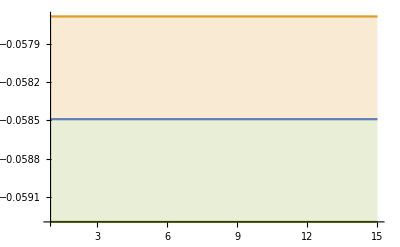

```mathematica
Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,15},Filling->{3->{1},2->{1}}]
```

```mathematica
SpoilHWFLOPlotN3=Show[Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,Length[meanErr2[[5]]]},Filling->{3->{1},2->{1}},PlotRange->{0,-.3}],ListPlot[{Table[{τSteps[[1,i]],meanErr2[[1,i]]},{i,1,Length[meanErr2[[1]]]}],Table[{τSteps[[2,i]],meanErr2[[2,i]]},{i,1,Length[meanErr2[[2]]]}],Table[{τSteps[[3,i]],meanErr2[[3,i]]},{i,1,Length[meanErr2[[3]]]}],Table[{τSteps[[4,i]],meanErr2[[4,i]]},{i,1,Length[meanErr2[[4]]]}],Table[{τSteps[[5,i]],meanErr2[[5,i]]},{i,1,Length[meanErr2[[5]]]}]},PlotRange->{-.03,-0.005},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]],markerlist[[4]],markerlist[[5]]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]},PlotStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau_{\\text{steps}}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3\\text{ (LO)}",Magnification->1.2]]
```

-Graphics-

#### QCD NLO - gauss

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={380,380,380,380,380};
NWalkers=200;
Nf4α1LoopBig={0.4,0.4,0.4,0.4,0.4};
aList={1,2,3,4,5};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
csvData=Table[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"],{xx,1,Length[aList]}]
```

({mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.268359255724612, -0.3016010545345508, -0.3071377342391511, -0.2335456394524169, -0.22667770524135486, -0.22880304565324178, -0.24126008455086614, -0.23237961043051847, -0.21650867997540363, -0.21630672369446755, -0.21824838767079296, -0.22259137288376943, -0.21801860782513183, -0.23903503735381168, -0.2320536551374768, -0.21346810638488845, -0.22909462299644373],[0.030087308384277964, 0.06406773023545802, 0.07369583254297514, 0.016280646354929422, 0.011837161319584193, 0.019670994765745298, 0.02085923645603082, 0.02463994574300341, 0.007993236862181076, 0.00865123372962971, 0.009621153402662022, 0.013496774874821404, 0.008949686626342525, 0.016627913300557386, 0.015987082119836647, 0.010563854838195922, 0.012763963763127183],-0.219248,0.00421985,1.13996}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.2243507069375273, -0.23331770321609716, -0.2804541192700164, -0.3629082379095484, -0.5562333686497374, -0.33816362037845576, -0.5887239046156109, -0.3795179729979453, -0.34612764909690497],[0.022373112746684333, 0.019294075370773517, 0.041844493735364946, 0.0966248663152598, 0.14687498135562216, 0.056384437169263286, 0.16230646571538257, 0.06930443255971937, 0.05042777061772786],-0.221832,0.601006,0.102839}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.21820754083936467, -0.24747631642967077, -0.20216036805422027, -0.1714293995340214, -0.19668076882580232, -0.22249266784247063, -0.40033214380339494, -0.22448877596786163],[0.024356890249749522, 0.04938461109169209, 0.016664275791303917, 0.014581585771980132, 0.020632194791462177, 0.057389810349133326, 0.19117152129111198, 0.04103821297802545],-0.184869,0.048473,0.776511}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.17260793879663666, -0.1846024077840137, -0.18854515278717815, -0.2070487616247927, -0.18896944422265577, -0.16530045335019336, -0.17155340490237989, -0.17538060489079066, -0.1880683333430665, -0.2180757874731673, -0.18696317979255586, -0.18036679214633342, -0.1820702210021649, -0.18259920870218255, -0.17721039282649423, -0.1827344849760755, -0.17173826105898818],[0.02966036290033275, 0.03670866731064433, 0.044986894663547244, 0.05773243936090824, 0.03723114254262139, 0.022989303488761447, 0.02647530205357634, 0.024663369719838374, 0.028434541450914327, 0.054614711458041955, 0.03230475766802257, 0.02302199056163053, 0.018894172240084328, 0.023951960484894636, 0.01600139973566323, 0.01820983642578582, 0.019538543106927018],-0.13869,0.00168089,0.489495}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.16503479580816574, -0.1753197667422637, -0.20689878091483482, -0.19188989779667898, -0.1625094267779284, -0.15402671983411637, -0.15639496982967413, -0.1848417825131755, -0.17289066868100383],[0.016905050630126272, 0.018336256084635818, 0.03839818411944776, 0.03414629985230969, 0.0207663248948761, 0.017813515510204925, 0.02004352396111691, 0.030340288800925957, 0.021042013174044465],-0.134335,0.00633276,0.924897})

```mathematica
meanErr=Table[Table[csvData[[xx,2,yy]]//StringSplit[#,{",","[","]"}]&,{yy,1,2}],{xx,1,Length[aList]}]
```

({-0.268359255724612, -0.3016010545345508, -0.3071377342391511, -0.2335456394524169, -0.22667770524135486, -0.22880304565324178, -0.24126008455086614, -0.23237961043051847, -0.21650867997540363, -0.21630672369446755, -0.21824838767079296, -0.22259137288376943, -0.21801860782513183, -0.23903503735381168, -0.2320536551374768, -0.21346810638488845, -0.22909462299644373} | {0.030087308384277964, 0.06406773023545802, 0.07369583254297514, 0.016280646354929422, 0.011837161319584193, 0.019670994765745298, 0.02085923645603082, 0.02463994574300341, 0.007993236862181076, 0.00865123372962971, 0.009621153402662022, 0.013496774874821404, 0.008949686626342525, 0.016627913300557386, 0.015987082119836647, 0.010563854838195922, 0.012763963763127183}
{-0.2243507069375273, -0.23331770321609716, -0.2804541192700164, -0.3629082379095484, -0.5562333686497374, -0.33816362037845576, -0.5887239046156109, -0.3795179729979453, -0.34612764909690497} | {0.022373112746684333, 0.019294075370773517, 0.041844493735364946, 0.0966248663152598, 0.14687498135562216, 0.056384437169263286, 0.16230646571538257, 0.06930443255971937, 0.05042777061772786}
{-0.21820754083936467, -0.24747631642967077, -0.20216036805422027, -0.1714293995340214, -0.19668076882580232, -0.22249266784247063, -0.40033214380339494, -0.22448877596786163} | {0.024356890249749522, 0.04938461109169209, 0.016664275791303917, 0.014581585771980132, 0.020632194791462177, 0.057389810349133326, 0.19117152129111198, 0.04103821297802545}
{-0.17260793879663666, -0.1846024077840137, -0.18854515278717815, -0.2070487616247927, -0.18896944422265577, -0.16530045335019336, -0.17155340490237989, -0.17538060489079066, -0.1880683333430665, -0.2180757874731673, -0.18696317979255586, -0.18036679214633342, -0.1820702210021649, -0.18259920870218255, -0.17721039282649423, -0.1827344849760755, -0.17173826105898818} | {0.02966036290033275, 0.03670866731064433, 0.044986894663547244, 0.05773243936090824, 0.03723114254262139, 0.022989303488761447, 0.02647530205357634, 0.024663369719838374, 0.028434541450914327, 0.054614711458041955, 0.03230475766802257, 0.02302199056163053, 0.018894172240084328, 0.023951960484894636, 0.01600139973566323, 0.01820983642578582, 0.019538543106927018}
{-0.16503479580816574, -0.1753197667422637, -0.20689878091483482, -0.19188989779667898, -0.1625094267779284, -0.15402671983411637, -0.15639496982967413, -0.1848417825131755, -0.17289066868100383} | {0.016905050630126272, 0.018336256084635818, 0.03839818411944776, 0.03414629985230969, 0.0207663248948761, 0.017813515510204925, 0.02004352396111691, 0.030340288800925957, 0.021042013174044465})

```mathematica
meanErr[[1,2,1]]//ToExpression
```

0.0300873

```mathematica
meanErr[[1]]
```

(-0.268359255724612 |  -0.3016010545345508 |  -0.3071377342391511 |  -0.2335456394524169 |  -0.22667770524135486 |  -0.22880304565324178 |  -0.24126008455086614 |  -0.23237961043051847 |  -0.21650867997540363 |  -0.21630672369446755 |  -0.21824838767079296 |  -0.22259137288376943 |  -0.21801860782513183 |  -0.23903503735381168 |  -0.2320536551374768 |  -0.21346810638488845 |  -0.22909462299644373
0.030087308384277964 |  0.06406773023545802 |  0.07369583254297514 |  0.016280646354929422 |  0.011837161319584193 |  0.019670994765745298 |  0.02085923645603082 |  0.02463994574300341 |  0.007993236862181076 |  0.00865123372962971 |  0.009621153402662022 |  0.013496774874821404 |  0.008949686626342525 |  0.016627913300557386 |  0.015987082119836647 |  0.010563854838195922 |  0.012763963763127183)

```mathematica
meanErr2=Table[Table[Around[meanErr[[xx,1,yy]]//ToExpression,meanErr[[xx,2,yy]]//ToExpression],{yy,1,Length[meanErr[[xx,1]]]}],{xx,1,Length[aList]}]
```

{{-0.2680.030,-0.300.06,-0.310.07,-0.2340.016,-0.2270.012,-0.2290.020,-0.2410.021,-0.2320.025,-0.2170.008,-0.2160.009,-0.2180.010,-0.2230.013,-0.2180.009,-0.2390.017,-0.2320.016,-0.2130.011,-0.2290.013},{-0.2240.022,-0.2330.019,-0.280.04,-0.360.10,-0.560.15,-0.340.06,-0.590.16,-0.380.07,-0.350.05},{-0.2180.024,-0.250.05,-0.2020.017,-0.1710.015,-0.1970.021,-0.220.06,-0.400.19,-0.220.04},{-0.1730.030,-0.180.04,-0.190.04,-0.210.06,-0.190.04,-0.1650.023,-0.1720.026,-0.1750.025,-0.1880.028,-0.220.05,-0.1870.032,-0.1800.023,-0.1820.019,-0.1830.024,-0.1770.016,-0.1830.018,-0.1720.020},{-0.1650.017,-0.1750.018,-0.210.04,-0.1920.034,-0.1630.021,-0.1540.018,-0.1560.020,-0.1850.030,-0.1730.021}}

```mathematica
τSteps=Table[Table[xx,{xx,1,Length[meanErr2[[yy]]]}],{yy,1,Length[meanErr2]}]
```

{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17},{1,2,3,4,5,6,7,8,9},{1,2,3,4,5,6,7,8},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17},{1,2,3,4,5,6,7,8,9}}

```mathematica
fitData=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"][[2,3]],Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"][[2,4]]],{xx,1,Length[aList]}]
```

{-0.2190.004,-0.20.6,-0.180.05,-0.13870.0017,-0.1340.006}

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][1]],{ii,5}],{MaTeX["a=1",Magnification->0.8],MaTeX["a=2",Magnification->0.8],MaTeX["a=3",Magnification->0.8],MaTeX["a=4",Magnification->0.8],MaTeX["a=5",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][3]],{ii,5}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

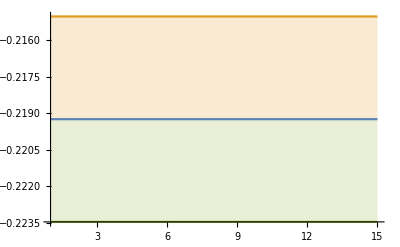

```mathematica
Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,15},Filling->{3->{1},2->{1}}]
```

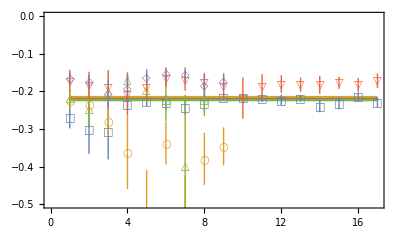

```mathematica
SpoilHWFLOPlotN3=Show[Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,Length[meanErr2[[4]]]},Filling->{3->{1},2->{1}},PlotRange->{-.5,0}],ListPlot[{Table[{τSteps[[1,i]],meanErr2[[1,i]]},{i,1,Length[meanErr2[[1]]]}],Table[{τSteps[[2,i]],meanErr2[[2,i]]},{i,1,Length[meanErr2[[2]]]}],Table[{τSteps[[3,i]],meanErr2[[3,i]]},{i,1,Length[meanErr2[[3]]]}],Table[{τSteps[[4,i]],meanErr2[[4,i]]},{i,1,Length[meanErr2[[4]]]}],Table[{τSteps[[5,i]],meanErr2[[5,i]]},{i,1,Length[meanErr2[[5]]]}]},PlotRange->{-.03,-0.005},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]],markerlist[[4]],markerlist[[5]]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]},PlotStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau_{\\text{steps}}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3(\\text{NLO})",Magnification->1.2]]
```

#### QCD mNLO - gauss

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={380,380,380,380,380};
NWalkers=200;
Nf4α1LoopBig={0.4,0.4,0.4,0.4,0.4};
aList={1,2,3,4,5};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
csvData=Table[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"],{xx,1,Length[aList]}]
```

({mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.19813521845756407, -0.18988538164891103, -0.21479382247969128, -0.19040157698240104, -0.19475732031953819, -0.19269949135956985, -0.19649839451289028, -0.2442703558552744, -0.30899015880832875, -0.45447400263157534, -0.4449283366457033, -0.8925828111763023, -0.6062874429398951, -0.4551259183170121, -0.40163325992157334, -0.31533020101798015, -0.4097909702700625, -0.40786415418723987, -0.22765753101298153, -0.19833684268166554, -0.18925427047514692, -0.190555327783366, -0.19642340055128973, -0.19531597482410476, -0.1975217758242388, -0.21476724866136954, -0.23839968445714294, -0.24466428494927628, -0.2646293066500764, -0.23430365852204163, -0.21242747784477495, -0.22642205751026148, -0.23050864832711251],[0.11262713900231809, 0.23245312479905195, 0.2790199803296923, 0.21674451556266802, 2.056725797900213, 1.459486381924022, 0.12160352703219583, 0.01084431500621132, 0.02747141697873977, 0.07464456064881324, 0.10425969694596354, 0.3054354235059035, 0.1579635085891896, 0.09264329300708485, 0.06737208035604382, 0.0376633338578225, 0.06332262812873705, 0.07680117555470885, 0.08077076897620739, 0.2520505222330573, 0.08205601026005825, 0.021456039821257832, 0.030802597007805573, 0.18376459602345202, 0.09018390992211771, 0.11039224811383982, 0.061448257765004476, 0.021214897927049902, 0.03578637069663333, 0.02680156485622922, 0.008299630874968503, 0.02542877333546403, 0.012915458104982682],-0.267224,1.40871,0.0155037}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.1740497192981142, -0.22017094474289173, -0.24928678472748728, -0.19860690866605935, -0.2283218718723256, -0.19570930987025542, -0.21894816547466364, -0.15595840956066687, -0.1818527904974106, -0.19083655512480965, -0.16560774906073797, -0.16052284692504853, -0.19266627524506807, -0.17934551550876948, -0.16842401937124846, -0.15294330708395298, -0.17711344380583843],[0.01157865492034962, 0.02437759517412726, 0.038610411141245915, 0.01925901746467855, 0.022485203363190168, 0.021137468323319836, 0.018598445411785684, 0.04665721484345231, 0.07144670158749312, 0.6246827063535227, 0.17946982979953302, 0.17360717159056463, 0.3124143359531371, 0.0690612249926316, 0.091099095988026, 0.12972652125840556, 0.1958232236659369],-0.285578,3.30975,0.0978213}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.2483018733014326, -0.24865080439060386, -0.29568128457814447, -0.2378662387705985, -0.3114329269254244, -0.3306789690796158, -0.36916584505649885, -0.5213160161551713, -0.43462910330439175, -0.47169522000897085, -0.32632826581200547, -0.3489928864431501, -0.3407736935145896, -0.2760916288787832, -0.21031538014542148, -0.20885486941787088, -0.2743910345007556],[0.046118051669082456, 0.05808742321902868, 0.13655232833485778, 0.05723648843760895, 0.10327954582637235, 0.08270394205964879, 0.24028504930021882, 0.16846179911646544, 0.11910373249716161, 0.130180021495288, 0.0752313034601387, 0.08189373357553714, 0.08458701078610838, 0.04975886287040104, 0.03809068935476566, 0.10239332380724915, 0.09665539030002414],-0.261527,3.06046,0.42523}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.37689253862451144, -0.3405998082769873, -0.45260156897059295, -0.5045902209113624, -0.5432635208342722, -0.47387720566889535, -0.6852727713893458, -0.3708367213284017, -0.405484700582985, -0.31868661707176843, -0.26536664317251224, -0.26123567681631277, -0.22477073004906062, -0.2373904425244938, -0.23697016392476064, -0.2572962612034162, -0.2912086680931666, -0.3470022840854115, -0.5826738359142242, -0.44251356537972586, -0.35941591099729275, -0.2804870725041279, -0.2743007041428713, -0.2639890680899399, -0.24458147595587534, -0.2199914785117625, -0.2005265192873626, -0.1951845768718244, -0.20838154247637458, -0.2673629749514684, -0.24377469656181194, -0.24080826137087466, -0.24146047717609964],[0.10977943236363474, 0.0904670407698952, 0.14234589924767058, 0.1699575159358374, 0.18825122726721427, 0.15333531596862712, 0.252344995739073, 0.10234584433352698, 0.11848334712226445, 0.07935674564760294, 0.05633837650351747, 0.05544454533077609, 0.03787049378244618, 0.04266630310840743, 0.03901155005126303, 0.04584585141626062, 0.06020043991083413, 0.08248482645192391, 0.19709346369075995, 0.12992743045081231, 0.09527286540024349, 0.056130860365515414, 0.05243496173501544, 0.047462997671588805, 0.03310221497602798, 0.02342244723991773, 0.0219914045556964, 0.023887796143562633, 0.01563421603536905, 0.04068710087464707, 0.029569741205300707, 0.030626910685572294, 0.03676764854897088],-0.24906,4.20725,0.0574708}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.1731219125089577, -0.19984661480173466, -0.1845767269838349, -0.20465002291296672, -0.21740922766381032, -0.23698437104996312, -0.1997315949265314, -0.19007243414024466, -0.16695477693370608, -0.16119183376507742, -0.15809115580748465, -0.15528786395159064, -0.15968997964683007, -0.17109324437933557, -0.19020940327225033, -0.1665590913576774, -0.17904839619465507],[0.018830197346084643, 0.02599034862566514, 0.020386988672040897, 0.030079160984489817, 0.04723612785695711, 0.062139691290686826, 0.041591285605906206, 0.02507613858430689, 0.024915962969330924, 0.02967273138912179, 0.02110397816782173, 0.024234606501188544, 0.023464962599764855, 0.02899507378124835, 0.035954642829362685, 0.02972329524147788, 0.02451996818089581],-0.163065,0.0047026,0.763889})

```mathematica
meanErr=Table[Table[csvData[[xx,2,yy]]//StringSplit[#,{",","[","]"}]&,{yy,1,2}],{xx,1,Length[aList]}]
```

({-0.19813521845756407, -0.18988538164891103, -0.21479382247969128, -0.19040157698240104, -0.19475732031953819, -0.19269949135956985, -0.19649839451289028, -0.2442703558552744, -0.30899015880832875, -0.45447400263157534, -0.4449283366457033, -0.8925828111763023, -0.6062874429398951, -0.4551259183170121, -0.40163325992157334, -0.31533020101798015, -0.4097909702700625, -0.40786415418723987, -0.22765753101298153, -0.19833684268166554, -0.18925427047514692, -0.190555327783366, -0.19642340055128973, -0.19531597482410476, -0.1975217758242388, -0.21476724866136954, -0.23839968445714294, -0.24466428494927628, -0.2646293066500764, -0.23430365852204163, -0.21242747784477495, -0.22642205751026148, -0.23050864832711251} | {0.11262713900231809, 0.23245312479905195, 0.2790199803296923, 0.21674451556266802, 2.056725797900213, 1.459486381924022, 0.12160352703219583, 0.01084431500621132, 0.02747141697873977, 0.07464456064881324, 0.10425969694596354, 0.3054354235059035, 0.1579635085891896, 0.09264329300708485, 0.06737208035604382, 0.0376633338578225, 0.06332262812873705, 0.07680117555470885, 0.08077076897620739, 0.2520505222330573, 0.08205601026005825, 0.021456039821257832, 0.030802597007805573, 0.18376459602345202, 0.09018390992211771, 0.11039224811383982, 0.061448257765004476, 0.021214897927049902, 0.03578637069663333, 0.02680156485622922, 0.008299630874968503, 0.02542877333546403, 0.012915458104982682}
{-0.1740497192981142, -0.22017094474289173, -0.24928678472748728, -0.19860690866605935, -0.2283218718723256, -0.19570930987025542, -0.21894816547466364, -0.15595840956066687, -0.1818527904974106, -0.19083655512480965, -0.16560774906073797, -0.16052284692504853, -0.19266627524506807, -0.17934551550876948, -0.16842401937124846, -0.15294330708395298, -0.17711344380583843} | {0.01157865492034962, 0.02437759517412726, 0.038610411141245915, 0.01925901746467855, 0.022485203363190168, 0.021137468323319836, 0.018598445411785684, 0.04665721484345231, 0.07144670158749312, 0.6246827063535227, 0.17946982979953302, 0.17360717159056463, 0.3124143359531371, 0.0690612249926316, 0.091099095988026, 0.12972652125840556, 0.1958232236659369}
{-0.2483018733014326, -0.24865080439060386, -0.29568128457814447, -0.2378662387705985, -0.3114329269254244, -0.3306789690796158, -0.36916584505649885, -0.5213160161551713, -0.43462910330439175, -0.47169522000897085, -0.32632826581200547, -0.3489928864431501, -0.3407736935145896, -0.2760916288787832, -0.21031538014542148, -0.20885486941787088, -0.2743910345007556} | {0.046118051669082456, 0.05808742321902868, 0.13655232833485778, 0.05723648843760895, 0.10327954582637235, 0.08270394205964879, 0.24028504930021882, 0.16846179911646544, 0.11910373249716161, 0.130180021495288, 0.0752313034601387, 0.08189373357553714, 0.08458701078610838, 0.04975886287040104, 0.03809068935476566, 0.10239332380724915, 0.09665539030002414}
{-0.37689253862451144, -0.3405998082769873, -0.45260156897059295, -0.5045902209113624, -0.5432635208342722, -0.47387720566889535, -0.6852727713893458, -0.3708367213284017, -0.405484700582985, -0.31868661707176843, -0.26536664317251224, -0.26123567681631277, -0.22477073004906062, -0.2373904425244938, -0.23697016392476064, -0.2572962612034162, -0.2912086680931666, -0.3470022840854115, -0.5826738359142242, -0.44251356537972586, -0.35941591099729275, -0.2804870725041279, -0.2743007041428713, -0.2639890680899399, -0.24458147595587534, -0.2199914785117625, -0.2005265192873626, -0.1951845768718244, -0.20838154247637458, -0.2673629749514684, -0.24377469656181194, -0.24080826137087466, -0.24146047717609964} | {0.10977943236363474, 0.0904670407698952, 0.14234589924767058, 0.1699575159358374, 0.18825122726721427, 0.15333531596862712, 0.252344995739073, 0.10234584433352698, 0.11848334712226445, 0.07935674564760294, 0.05633837650351747, 0.05544454533077609, 0.03787049378244618, 0.04266630310840743, 0.03901155005126303, 0.04584585141626062, 0.06020043991083413, 0.08248482645192391, 0.19709346369075995, 0.12992743045081231, 0.09527286540024349, 0.056130860365515414, 0.05243496173501544, 0.047462997671588805, 0.03310221497602798, 0.02342244723991773, 0.0219914045556964, 0.023887796143562633, 0.01563421603536905, 0.04068710087464707, 0.029569741205300707, 0.030626910685572294, 0.03676764854897088}
{-0.1731219125089577, -0.19984661480173466, -0.1845767269838349, -0.20465002291296672, -0.21740922766381032, -0.23698437104996312, -0.1997315949265314, -0.19007243414024466, -0.16695477693370608, -0.16119183376507742, -0.15809115580748465, -0.15528786395159064, -0.15968997964683007, -0.17109324437933557, -0.19020940327225033, -0.1665590913576774, -0.17904839619465507} | {0.018830197346084643, 0.02599034862566514, 0.020386988672040897, 0.030079160984489817, 0.04723612785695711, 0.062139691290686826, 0.041591285605906206, 0.02507613858430689, 0.024915962969330924, 0.02967273138912179, 0.02110397816782173, 0.024234606501188544, 0.023464962599764855, 0.02899507378124835, 0.035954642829362685, 0.02972329524147788, 0.02451996818089581})

```mathematica
meanErr[[1,2,1]]//ToExpression
```

0.112627

```mathematica
meanErr[[1]]
```

(-0.19813521845756407 |  -0.18988538164891103 |  -0.21479382247969128 |  -0.19040157698240104 |  -0.19475732031953819 |  -0.19269949135956985 |  -0.19649839451289028 |  -0.2442703558552744 |  -0.30899015880832875 |  -0.45447400263157534 |  -0.4449283366457033 |  -0.8925828111763023 |  -0.6062874429398951 |  -0.4551259183170121 |  -0.40163325992157334 |  -0.31533020101798015 |  -0.4097909702700625 |  -0.40786415418723987 |  -0.22765753101298153 |  -0.19833684268166554 |  -0.18925427047514692 |  -0.190555327783366 |  -0.19642340055128973 |  -0.19531597482410476 |  -0.1975217758242388 |  -0.21476724866136954 |  -0.23839968445714294 |  -0.24466428494927628 |  -0.2646293066500764 |  -0.23430365852204163 |  -0.21242747784477495 |  -0.22642205751026148 |  -0.23050864832711251
0.11262713900231809 |  0.23245312479905195 |  0.2790199803296923 |  0.21674451556266802 |  2.056725797900213 |  1.459486381924022 |  0.12160352703219583 |  0.01084431500621132 |  0.02747141697873977 |  0.07464456064881324 |  0.10425969694596354 |  0.3054354235059035 |  0.1579635085891896 |  0.09264329300708485 |  0.06737208035604382 |  0.0376633338578225 |  0.06332262812873705 |  0.07680117555470885 |  0.08077076897620739 |  0.2520505222330573 |  0.08205601026005825 |  0.021456039821257832 |  0.030802597007805573 |  0.18376459602345202 |  0.09018390992211771 |  0.11039224811383982 |  0.061448257765004476 |  0.021214897927049902 |  0.03578637069663333 |  0.02680156485622922 |  0.008299630874968503 |  0.02542877333546403 |  0.012915458104982682)

```mathematica
meanErr2=Table[Table[Around[meanErr[[xx,1,yy]]//ToExpression,meanErr[[xx,2,yy]]//ToExpression],{yy,1,Length[meanErr[[xx,1]]]}],{xx,1,Length[aList]}]
```

{{-0.200.11,-0.190.23,-0.210.28,-0.190.22,-0.22.1,-0.21.5,-0.200.12,-0.2440.011,-0.3090.027,-0.450.07,-0.440.10,-0.890.31,-0.610.16,-0.460.09,-0.400.07,-0.320.04,-0.410.06,-0.410.08,-0.230.08,-0.200.25,-0.190.08,-0.1910.021,-0.1960.031,-0.200.18,-0.200.09,-0.210.11,-0.240.06,-0.2450.021,-0.260.04,-0.2340.027,-0.2120.008,-0.2260.025,-0.2310.013},{-0.1740.012,-0.2200.024,-0.250.04,-0.1990.019,-0.2280.022,-0.1960.021,-0.2190.019,-0.160.05,-0.180.07,-0.20.6,-0.170.18,-0.160.17,-0.190.31,-0.180.07,-0.170.09,-0.150.13,-0.180.20},{-0.250.05,-0.250.06,-0.300.14,-0.240.06,-0.310.10,-0.330.08,-0.370.24,-0.520.17,-0.430.12,-0.470.13,-0.330.08,-0.350.08,-0.340.08,-0.280.05,-0.210.04,-0.210.10,-0.270.10},{-0.380.11,-0.340.09,-0.450.14,-0.500.17,-0.540.19,-0.470.15,-0.690.25,-0.370.10,-0.410.12,-0.320.08,-0.270.06,-0.260.06,-0.220.04,-0.240.04,-0.240.04,-0.260.05,-0.290.06,-0.350.08,-0.580.20,-0.440.13,-0.360.10,-0.280.06,-0.270.05,-0.260.05,-0.2450.033,-0.2200.023,-0.2010.022,-0.1950.024,-0.2080.016,-0.270.04,-0.2440.030,-0.2410.031,-0.240.04},{-0.1730.019,-0.2000.026,-0.1850.020,-0.2050.030,-0.220.05,-0.240.06,-0.200.04,-0.1900.025,-0.1670.025,-0.1610.030,-0.1580.021,-0.1550.024,-0.1600.023,-0.1710.029,-0.190.04,-0.1670.030,-0.1790.025}}

```mathematica
τSteps=Table[Table[xx,{xx,1,Length[meanErr2[[yy]]]}],{yy,1,Length[meanErr2]}]
```

{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17}}

```mathematica
fitData=Table[Around[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"][[2,3]],Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"][[2,4]]],{xx,1,Length[aList]}]
```

{-0.31.4,-0.33.3,-0.33.1,0.4.,-0.1630.005}

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][1]],{ii,5}],{MaTeX["a=1",Magnification->0.8],MaTeX["a=2",Magnification->0.8],MaTeX["a=3",Magnification->0.8],MaTeX["a=4",Magnification->0.8],MaTeX["a=5",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][3]],{ii,5}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

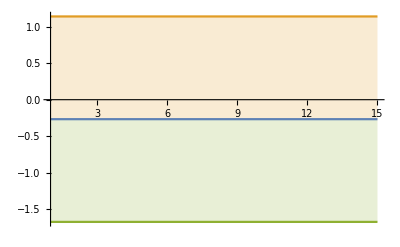

```mathematica
Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,15},Filling->{3->{1},2->{1}}]
```

```mathematica
SpoilHWFLOPlotN3=Show[Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,Length[meanErr2[[5]]]},Filling->{3->{1},2->{1}},PlotRange->{-.5,0}],ListPlot[{Table[{τSteps[[1,i]],meanErr2[[1,i]]},{i,1,Length[meanErr2[[1]]]}],Table[{τSteps[[2,i]],meanErr2[[2,i]]},{i,1,Length[meanErr2[[2]]]}],Table[{τSteps[[3,i]],meanErr2[[3,i]]},{i,1,Length[meanErr2[[3]]]}],Table[{τSteps[[4,i]],meanErr2[[4,i]]},{i,1,Length[meanErr2[[4]]]}],Table[{τSteps[[5,i]],meanErr2[[5,i]]},{i,1,Length[meanErr2[[5]]]}]},PlotRange->{-.1,-0.005},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]],markerlist[[4]],markerlist[[5]]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]},PlotStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau_{\\text{steps}}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3(\\text{mNLO})",Magnification->1.2]]
```

-Graphics-

#### QCD NNLO - gauss

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={393,393,393,393,393};
NWalkers=200;
Nf4α1LoopBig={0.4,0.4,0.4,0.4,0.4};
aList={1,2,3,4,5};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
csvData=Table[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"],{xx,1,Length[aList]}]
```

({mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.6033159069210966, -0.7278500141899154, -0.7942217516020047, -0.6712532793840992, -0.5757526876515683, -0.6294032090035531, -0.5109052632870709, -0.5669972521578669, -0.5295706366275719],[0.03803162893044689, 0.13061172698412624, 0.18175674342154993, 0.10838118102315956, 0.04341423438326216, 0.052054226001975144, 0.029581482194788913, 0.03377632606246855, 0.021560880410255227],-0.540162,0.0070678,1.45796}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.44276701181003847, -0.42416739715136215, -0.47035599129675054, -0.47963314742462354, -0.46611444716093314, -0.5537297133754118, -0.5485060164278885, -0.48583208213701756, -0.46990156388287835],[0.0586894055631927, 0.04940196710435787, 0.1640207823856441, 0.15160943792925416, 0.09382571633941754, 0.13345559868321077, 0.12798824869253864, 0.06843396746572877, 0.08747935230902824],-0.480539,0.721284,0.330329}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.48984367136865686, -0.4796781136423196, -0.494026382439559, -0.44207200849681566, -0.41922514806357286, -0.4168797223416276, -0.44440747664055313, -0.4823143451711152, -0.4564852096993456, -0.4366920297340906, -0.44374523449327735, -0.4264551513324604, -0.4163938975198974, -0.43981632520077946, -0.41935868424974665, -0.4301376965735393, -0.4048063916495993],[0.07284807406784034, 0.053032692687421834, 0.03312274041671284, 0.059501167358997124, 0.08499781772094928, 0.09393610393286607, 0.0716105846150971, 0.05158762263751556, 0.08483085204151007, 0.08173609008965856, 0.10504316762730813, 0.14981768416234276, 0.09231300575616408, 0.05555632273195881, 0.05662386306997431, 0.06337821220123928, 0.058026473331926585],-0.484926,1.39557,0.00593785}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.31235242061018564, -0.3300634812696686, -0.3516087346039349],[0.0498507037576001, 0.048189627628361, 0.040598412739080436],-0.394649,0.00868448,0.880562}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.3479103797650722, -0.3320259609486495, -0.32278319700708474, -0.3289265656618109, -0.3099553330164854, -0.3106532101734212, -0.3123790755845816, -0.31069152986970233, -0.31492522590035776, -0.33999451806105185, -0.33991263987194786, -0.3365622949524513, -0.3384701766920318, -0.34423211273077187, -0.33752934027872683, -0.3405590515968915, -0.34809592841520565],[0.04026261702055909, 0.07960413531889576, 0.07099253744730995, 0.10993451607969498, 0.07431191459523317, 0.0873885165878948, 0.09460096701636105, 0.0822737400112141, 0.08987894881915677, 0.08510371792696496, 0.07010881464102578, 0.07180262458302943, 0.07769401055746504, 0.07760798473027962, 0.08435983828216873, 0.078222658300063, 0.07362252137746778],-0.382246,1.48218,0.00558994})

```mathematica
meanErr=Table[Table[csvData[[xx,2,yy]]//StringSplit[#,{",","[","]"}]&,{yy,1,2}],{xx,1,Length[aList]}]
```

({-0.6033159069210966, -0.7278500141899154, -0.7942217516020047, -0.6712532793840992, -0.5757526876515683, -0.6294032090035531, -0.5109052632870709, -0.5669972521578669, -0.5295706366275719} | {0.03803162893044689, 0.13061172698412624, 0.18175674342154993, 0.10838118102315956, 0.04341423438326216, 0.052054226001975144, 0.029581482194788913, 0.03377632606246855, 0.021560880410255227}
{-0.44276701181003847, -0.42416739715136215, -0.47035599129675054, -0.47963314742462354, -0.46611444716093314, -0.5537297133754118, -0.5485060164278885, -0.48583208213701756, -0.46990156388287835} | {0.0586894055631927, 0.04940196710435787, 0.1640207823856441, 0.15160943792925416, 0.09382571633941754, 0.13345559868321077, 0.12798824869253864, 0.06843396746572877, 0.08747935230902824}
{-0.48984367136865686, -0.4796781136423196, -0.494026382439559, -0.44207200849681566, -0.41922514806357286, -0.4168797223416276, -0.44440747664055313, -0.4823143451711152, -0.4564852096993456, -0.4366920297340906, -0.44374523449327735, -0.4264551513324604, -0.4163938975198974, -0.43981632520077946, -0.41935868424974665, -0.4301376965735393, -0.4048063916495993} | {0.07284807406784034, 0.053032692687421834, 0.03312274041671284, 0.059501167358997124, 0.08499781772094928, 0.09393610393286607, 0.0716105846150971, 0.05158762263751556, 0.08483085204151007, 0.08173609008965856, 0.10504316762730813, 0.14981768416234276, 0.09231300575616408, 0.05555632273195881, 0.05662386306997431, 0.06337821220123928, 0.058026473331926585}
{-0.31235242061018564, -0.3300634812696686, -0.3516087346039349} | {0.0498507037576001, 0.048189627628361, 0.040598412739080436}
{-0.3479103797650722, -0.3320259609486495, -0.32278319700708474, -0.3289265656618109, -0.3099553330164854, -0.3106532101734212, -0.3123790755845816, -0.31069152986970233, -0.31492522590035776, -0.33999451806105185, -0.33991263987194786, -0.3365622949524513, -0.3384701766920318, -0.34423211273077187, -0.33752934027872683, -0.3405590515968915, -0.34809592841520565} | {0.04026261702055909, 0.07960413531889576, 0.07099253744730995, 0.10993451607969498, 0.07431191459523317, 0.0873885165878948, 0.09460096701636105, 0.0822737400112141, 0.08987894881915677, 0.08510371792696496, 0.07010881464102578, 0.07180262458302943, 0.07769401055746504, 0.07760798473027962, 0.08435983828216873, 0.078222658300063, 0.07362252137746778})

```mathematica
meanErr2=Table[Table[Around[meanErr[[xx,1,yy]]//ToExpression,meanErr[[xx,2,yy]]//ToExpression],{yy,1,Length[meanErr[[xx,1]]]}],{xx,1,Length[aList]}]
```

{{-0.600.04,-0.730.13,-0.790.18,-0.670.11,-0.580.04,-0.630.05,-0.5110.030,-0.5670.034,-0.5300.022},{-0.440.06,-0.420.05,-0.470.16,-0.480.15,-0.470.09,-0.550.13,-0.550.13,-0.490.07,-0.470.09},{-0.490.07,-0.480.05,-0.4940.033,-0.440.06,-0.420.08,-0.420.09,-0.440.07,-0.480.05,-0.460.08,-0.440.08,-0.440.11,-0.430.15,-0.420.09,-0.440.06,-0.420.06,-0.430.06,-0.400.06},{-0.310.05,-0.330.05,-0.350.04},{-0.350.04,-0.330.08,-0.320.07,-0.330.11,-0.310.07,-0.310.09,-0.310.09,-0.310.08,-0.310.09,-0.340.09,-0.340.07,-0.340.07,-0.340.08,-0.340.08,-0.340.08,-0.340.08,-0.350.07}}

```mathematica
τSteps=Table[Table[xx,{xx,1,Length[meanErr2[[yy]]]}],{yy,1,Length[meanErr2]}]
```

{{1,2,3,4,5,6,7,8,9},{1,2,3,4,5,6,7,8,9},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17},{1,2,3},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17}}

```mathematica
fitData=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"][[2,3]],Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"][[2,4]]],{xx,1,Length[aList]}]
```

{-0.5400.007,-0.50.7,-0.51.4,-0.3950.009,-0.41.5}

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][1]],{ii,5}],{MaTeX["a=1",Magnification->0.8],MaTeX["a=2",Magnification->0.8],MaTeX["a=3",Magnification->0.8],MaTeX["a=4",Magnification->0.8],MaTeX["a=5",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][3]],{ii,5}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

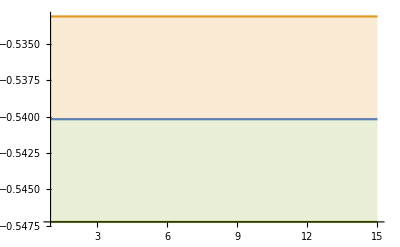

```mathematica
Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,15},Filling->{3->{1},2->{1}}]
```

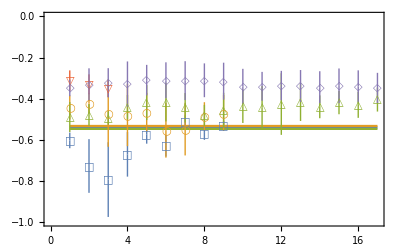

```mathematica
SpoilHWFLOPlotN3=Show[Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,Length[meanErr2[[5]]]},Filling->{3->{1},2->{1}},PlotRange->{-1,0}],ListPlot[{Table[{τSteps[[1,i]],meanErr2[[1,i]]},{i,1,Length[meanErr2[[1]]]}],Table[{τSteps[[2,i]],meanErr2[[2,i]]},{i,1,Length[meanErr2[[2]]]}],Table[{τSteps[[3,i]],meanErr2[[3,i]]},{i,1,Length[meanErr2[[3]]]}],Table[{τSteps[[4,i]],meanErr2[[4,i]]},{i,1,Length[meanErr2[[4]]]}],Table[{τSteps[[5,i]],meanErr2[[5,i]]},{i,1,Length[meanErr2[[5]]]}]},PlotRange->{-.1,-0.005},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]],markerlist[[4]],markerlist[[5]]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]},PlotStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau_{\\text{steps}}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3(\\text{NNLO})",Magnification->1.2]]
```

## Baryons

### a=0.2 dτ=0.2

#### QCD LO - HWF

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={430,430,430,430,430};
NWalkers=200;
Nf4α1LoopBig={0.21556,0.21556,0.21556,0.21556,0.21556};
aList={1,2,3,4,5};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
csvData=Table[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"],{xx,1,Length[aList]}]
```

({mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.022235321554132596, -0.022234097582423715, -0.022235098815838142, -0.02223290377236056, -0.022236512680626905, -0.022253450237932036, -0.02224982587450169, -0.022250243640036138, -0.02225192936908661, -0.022243288307061924, -0.022239671562506867, -0.02223655820250948, -0.02222399260722786, -0.022212746134845356, -0.022205476005924187, -0.022214739859178097, -0.022214713295324148, -0.02218797061487831, -0.02218548426618348, -0.022170624423476424, -0.022165562565845853, -0.022169506099150506, -0.02217084121322459, -0.022185018383319658, -0.022179783883372852, -0.022181430245340646, -0.02218351935130233, -0.02217723886012841, -0.022169526682932983, -0.02217032733244699, -0.02213287711667591, -0.022135874772240258, -0.022142977554498053, -0.0221380294878606, -0.02213813993187805, -0.022126610119184462, -0.02213318022613961, -0.02211346958735632, -0.02211456730413212, -0.02211686866009868, -0.022107892144713457, -0.02210245052312838, -0.022115963051651182, -0.022122534930259334, -0.022129561545933384, -0.022124679648589784, -0.02210997264665743, -0.02210441150884744, -0.022111340063416664, -0.02209990912346145, -0.022098296929646516, -0.02207382846916216, -0.022078777610756637, -0.022073099190205066, -0.022057110342809664, -0.02205482420491917, -0.02207674211798214, -0.022081167809771086, -0.02208064515235488, -0.022074580448549208, -0.022060631229515276, -0.022063967311420882, -0.02207681143101776, -0.022086600437016473, -0.022075565300687713, -0.02206498602591417, -0.022060678449815525, -0.022050688604761472, -0.022056239295669626, -0.022046010183871884, -0.02206904086438001, -0.02208287559980716, -0.02208076109482079, -0.02211173191889907, -0.022111493576556625, -0.022123132411391695, -0.02211229632097493, -0.0221206181238669, -0.022142912834884787, -0.022147579993577696, -0.02214993703586355, -0.022146439763039313, -0.022143494337453516, -0.02214651380359175, -0.022133243090265937, -0.02213836848914944, -0.02214416585666949, -0.02214055382218544, -0.022137912434293278, -0.022128518444254425, -0.02211533643466543, -0.022117109736099927, -0.022150058763669895, -0.022129227188471687, -0.022141699968134077, -0.02212744950780144, -0.02213994000642706, -0.022143315406211627, -0.02216438470690059, -0.022187581337469106, -0.022172271026044202, -0.022161784975424616, -0.02216317156461272, -0.0221538363086458, -0.02214148029652, -0.022125436547321933, -0.0221158114607796, -0.022104576251289587, -0.022092740120715555, -0.022082359427912947, -0.02208396719373647, -0.022086601729803576, -0.022084872078239077, -0.022115699168083716, -0.022116873496148597, -0.022117480373377945, -0.02212190433170086, -0.022111216535007226, -0.02210989930065779, -0.022109534334476114, -0.02212120298651442, -0.02211537228988246, -0.022118757930677448, -0.02212568000872423, -0.02213353372285638, -0.022148771147062138, -0.02214898928280308, -0.022161557473106403, -0.022165605013627434, -0.022166694091409294, -0.02217731518603383, -0.022173394835309786, -0.02215494868541347, -0.022138661865528975, -0.022155765372953762, -0.022128588681638646, -0.02212996719839274, -0.02212695208196238, -0.022120742124075415, -0.02210087496243391, -0.022128294546959137, -0.02213319053101107, -0.022146171445709985, -0.022139480943237824, -0.02214420895592995, -0.022145193321823187, -0.02214007394005381, -0.022141538022494158, -0.022141361620774923, -0.02214722469706339, -0.02214790831137147, -0.022142955563528913, -0.022131721120451312, -0.02212861088871109, -0.02212170998475112, -0.022140794761174535, -0.02212786491599748, -0.022120300426955373, -0.022124284194816442, -0.022144319110255224, -0.022162541159635528, -0.022148591012221552, -0.022130215623773673, -0.022146904151687314, -0.022142262720549283, -0.022131371909796693, -0.022154514532612534, -0.022140521553640897, -0.02214324982559318, -0.02213760008041701, -0.022143704645566125, -0.02216682803313127, -0.022166922461367002, -0.022158573509254514, -0.022143424146743675, -0.022147830927218354, -0.022151054113058597, -0.022153494149446354, -0.02213927460633258, -0.02213837773449527, -0.022129991421993567, -0.02213252641629489, -0.022133931529029906, -0.02214045591978435, -0.02212818853767251, -0.022126218488319045, -0.022121511779802, -0.02213656092039754, -0.02215082371355544, -0.022144556646252173, -0.022134054536483382, -0.02214569286731265, -0.022156666500382862, -0.02214247765007109, -0.022153227264032165, -0.022146021339668757, -0.02215057469319718, -0.022141642565740787, -0.022139309947850315, -0.022122058720126802, -0.022109511125857326, -0.022115403076116612, -0.022105033453446925, -0.02212115680471444, -0.022105790782998243, -0.0221152274649192, -0.022112220866397178, -0.022127479030090654, -0.02212495348668277, -0.022129343158814718, -0.02212315294407663, -0.022119172705319906, -0.022113841375931687, -0.02211359259540474, -0.022102444368682857, -0.02211024425892245, -0.022113345644517647, -0.022116644173721844, -0.022133183284498776, -0.022122921423349397, -0.02212657186031311, -0.022124316105027683, -0.022126891245954294, -0.02213417546681931, -0.022128363972885888, -0.022113454895794353, -0.022126969904720063, -0.02214134633485212, -0.02212580313143883, -0.02214301442100001, -0.022146387607632868, -0.02215592268984515, -0.02215524241603887, -0.02215451296070193, -0.02214434036329389, -0.0221363730611001, -0.02212141598655206, -0.022107146484646085, -0.022114554139619276, -0.02210572911999652, -0.022113591835736017, -0.02213824842277202, -0.02210565919487252, -0.022104232731496948, -0.022079049610174217, -0.02208919044232936, -0.022097386617263706, -0.022086152166935363, -0.022097280111521584, -0.022093013008003363, -0.022066913974355132, -0.0220700002329891, -0.02205716457788545, -0.022065670502875435, -0.02207452200944819, -0.022067484135875736, -0.022077750903740524, -0.022091764812332795, -0.022083425500798504, -0.02209262749465288, -0.022096243458573066, -0.02210644244651232, -0.022087743616102877, -0.022098408236053354, -0.022098870614093696, -0.022096326950191446, -0.02210034681223649, -0.02210805999218903, -0.02209853423971195, -0.02209934472055128, -0.02209938586517994, -0.022092092181854994, -0.02207298560571093, -0.022084628643657272, -0.022112390983342157, -0.02210941273519816, -0.022130326720201515],[4.4621672811155705e-05, 4.741342664131019e-05, 4.784547957180435e-05, 4.77817304205791e-05, 4.777330664664324e-05, 4.6194197436616107e-05, 4.670844705284097e-05, 4.634543359873657e-05, 4.7153864377003066e-05, 4.688836602279486e-05, 4.75395689046464e-05, 4.905540844363217e-05, 4.978478617876505e-05, 4.985843529949984e-05, 5.049091557181565e-05, 4.9613603606976583e-05, 4.86274512942933e-05, 4.905500572670624e-05, 4.897445305385418e-05, 4.909685493238634e-05, 5.008752475620751e-05, 4.874224733124864e-05, 4.887832872701955e-05, 4.868441277814083e-05, 4.9506517773183036e-05, 4.848748305171356e-05, 4.803494027325932e-05, 4.922785822960143e-05, 4.9430182702038e-05, 4.962492550731265e-05, 4.9460530537783916e-05, 4.96493695939955e-05, 5.1077743858414425e-05, 5.221419842820509e-05, 5.2945189842320475e-05, 5.323298569325509e-05, 5.19489812581722e-05, 5.392615128567533e-05, 5.354643946386612e-05, 5.1620656793293564e-05, 5.043721172908672e-05, 4.9749971450375296e-05, 5.138454668247647e-05, 5.0545113925390367e-05, 4.9913470492515385e-05, 4.672562140925508e-05, 4.865512453144245e-05, 4.7926345588728656e-05, 4.712060238398105e-05, 4.7816999781003785e-05, 4.765779870694743e-05, 5.0015024636329165e-05, 5.26347256352005e-05, 5.304667366144572e-05, 5.3013857699558114e-05, 5.3297469848476696e-05, 5.31576663829709e-05, 5.1872747279708024e-05, 5.253146840836686e-05, 5.220280455219635e-05, 5.209537682264667e-05, 5.3996716152664564e-05, 5.556477558387775e-05, 5.6044679522316346e-05, 5.654359758715237e-05, 5.607131834037077e-05, 5.5291519514054446e-05, 5.6000172079822565e-05, 5.557559978795719e-05, 5.623324865084916e-05, 5.6538521434764155e-05, 5.5985600216151364e-05, 5.614190177810256e-05, 5.450542916723273e-05, 5.484245494985952e-05, 5.4496800941878116e-05, 5.352737874531642e-05, 5.283093405949696e-05, 5.3391393226341894e-05, 5.394116863161818e-05, 5.173144686063554e-05, 5.180515300740948e-05, 5.177125322521927e-05, 5.108480660500577e-05, 4.965310466786031e-05, 4.5971733940704596e-05, 4.449030161561114e-05, 4.462747827111207e-05, 4.2717420805014414e-05, 4.1608681417546594e-05, 4.3072474320396e-05, 4.3018386711560215e-05, 4.404000875027771e-05, 4.3958548816965555e-05, 4.30646413690288e-05, 4.344754029071974e-05, 4.368471877689297e-05, 4.366142436170308e-05, 4.3728983604558966e-05, 4.250369043722506e-05, 4.3205562140985417e-05, 4.109035955660951e-05, 4.204397790330984e-05, 4.330726440559539e-05, 4.298515720068025e-05, 4.405015756001645e-05, 4.528675752788657e-05, 4.4041552656611786e-05, 4.398636365081034e-05, 4.5267668233719036e-05, 4.647870094643143e-05, 4.824544146106265e-05, 4.712650809286435e-05, 4.823078354656058e-05, 4.9147382926406e-05, 4.910524114246179e-05, 4.7341881951138036e-05, 4.618165816236599e-05, 4.543100206969094e-05, 4.8232772330403274e-05, 4.909233116215578e-05, 4.982307898906626e-05, 5.141302311918941e-05, 4.9086693818900394e-05, 4.714513122923747e-05, 4.861409990094735e-05, 4.8775703730281385e-05, 4.779923749523163e-05, 4.818111551097592e-05, 5.010646861731168e-05, 4.8068660559794764e-05, 4.8194362394750506e-05, 4.915026352340679e-05, 5.039958940056621e-05, 4.9870680393237955e-05, 5.30430574374579e-05, 5.339808182208744e-05, 5.1484807738872645e-05, 5.3526807048806746e-05, 5.390017051706832e-05, 5.1821107602598304e-05, 5.286154003987178e-05, 5.2029248982503715e-05, 5.120960473437121e-05, 5.182905577149733e-05, 5.0638432838633945e-05, 4.994072155028548e-05, 5.103286104554708e-05, 5.0116471462630674e-05, 4.86861067060587e-05, 4.868656162628134e-05, 4.813587381812168e-05, 4.9028864753647364e-05, 4.72805365007688e-05, 4.812750645586759e-05, 4.6707907893955835e-05, 4.72452742422409e-05, 4.7818009308670746e-05, 4.67596329611653e-05, 4.5643836694306093e-05, 4.54272815399801e-05, 4.75527122944713e-05, 4.7177623316342706e-05, 4.5035173591609794e-05, 4.664431567652211e-05, 4.561291150794528e-05, 4.6159907922832764e-05, 4.777468007759145e-05, 4.818072516552902e-05, 4.6610017883027046e-05, 4.8086028928586774e-05, 4.665748006570177e-05, 4.7035112011419724e-05, 4.732747020759252e-05, 4.6962786627034834e-05, 4.57366348116934e-05, 4.747636441310972e-05, 4.79748166449173e-05, 4.8938527560588244e-05, 4.789712029732623e-05, 4.885673891227264e-05, 4.894428862644033e-05, 5.0010026512882476e-05, 5.045456457369515e-05, 5.181795615349233e-05, 5.199111704415026e-05, 5.113600644077365e-05, 4.957740907625783e-05, 5.024772528369153e-05, 5.026197328032869e-05, 5.127823398775441e-05, 5.031546730671406e-05, 4.992574779588268e-05, 5.04177297394795e-05, 5.094726165173023e-05, 4.969056538542294e-05, 4.986516727218579e-05, 4.901458889763818e-05, 4.910383982403499e-05, 4.7495354804883693e-05, 4.8158149796078965e-05, 4.711299748810848e-05, 4.6618641594921925e-05, 4.797275155000845e-05, 4.73321485736514e-05, 4.8690935883966004e-05, 5.058546882036501e-05, 4.94332792972178e-05, 5.082755985395095e-05, 5.068009116624369e-05, 5.3131339452036226e-05, 5.186440636926196e-05, 4.980774476389592e-05, 5.123392460144664e-05, 5.0796357453189145e-05, 4.992122182576723e-05, 5.0723517173288836e-05, 5.029029421996439e-05, 4.8936913097255535e-05, 4.893221479717305e-05, 5.0489954397924586e-05, 4.915332409675303e-05, 4.938056607035777e-05, 4.8573845010887405e-05, 4.9689280738432045e-05, 5.041768483852383e-05, 5.110182926975335e-05, 5.2295048553265724e-05, 5.432223633507794e-05, 5.334444097149857e-05, 5.3233672832187416e-05, 5.224904776535864e-05, 5.1485505292921416e-05, 5.011760064813557e-05, 5.1792053843431044e-05, 5.29370021193981e-05, 5.426727011305007e-05, 5.3291178640954434e-05, 5.423013184034926e-05, 5.4968884578864204e-05, 5.430137716636157e-05, 5.395905395218368e-05, 5.548299831528914e-05, 5.340028428619603e-05, 5.512176545229134e-05, 5.6174974134552904e-05, 5.4323594607116265e-05, 5.297917759888602e-05, 5.184034243548263e-05, 5.097768392420073e-05, 5.216081389828991e-05, 5.2119212395164966e-05, 5.1115913949907814e-05, 5.065350140771788e-05, 5.201082295786338e-05, 5.199545982755747e-05, 5.257725146410657e-05, 5.2010598669137354e-05, 5.212486291800645e-05, 5.18976080641184e-05, 5.1274391412389714e-05, 4.895828074970701e-05, 5.1260676576026887e-05, 4.913020889644418e-05, 4.88821058191325e-05, 4.9189257688059624e-05, 4.964138145009273e-05, 5.071900990749255e-05, 5.031124467859978e-05, 5.095519287000467e-05, 5.1271265494238964e-05, 5.3670049623267104e-05, 5.435593012637632e-05, 5.501849447670744e-05, 5.353217430504901e-05, 5.629230769704516e-05, 5.5905037275088744e-05],-0.0221355,0.000013934,1.48797}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.01681793631624839, -0.017095735967840246, -0.016869479985142204, -0.01692624760591709, -0.0169290624145117, -0.016868269259655528, -0.016972518713458205, -0.016983943186392837, -0.01700171913872897, -0.017120649975551724, -0.01711850288877605, -0.01695820211261302, -0.017029882269379647, -0.017254543888388756, -0.01709154758237453, -0.016946980430602384, -0.017318608470528983, -0.01723460229060472, -0.01725230460112511, -0.01726997804916964, -0.017440167432464265, -0.017164525738601548, -0.017207814916240266, -0.017332937928972125, -0.01734490711462931, -0.017458547448117253, -0.017451350374259454, -0.01744270068578619, -0.017433522826318566, -0.017454750765077267, -0.017465368657580086, -0.017305483180096073, -0.017255925496187183, -0.017179524047900338, -0.017325343635966425, -0.017255725269903262, -0.01732735327363226, -0.017198614150266422, -0.017313197972986364, -0.017240963267981822, -0.017264806782210398, -0.01716768731053712, -0.01723824701086612, -0.017367507624485235, -0.017396454937181522, -0.01733483394117522, -0.01729866010733002, -0.017794235780344548, -0.01721793813136116, -0.016925210027611437, -0.016933104620724403, -0.01702307263601021, -0.016783805268334704, -0.016900206786360637, -0.016985086569275786, -0.01718291014213668, -0.017531268632445886, -0.017085084969614642, -0.017032982425470234, -0.01692166059920625, -0.01708262279584945, -0.01718715212898265, -0.017269276534811136, -0.017287084710925084, -0.01712729635545565, -0.016954836073468923, -0.017032661820031582, -0.017001455951233535, -0.01692639758469943, -0.016918688709308564, -0.01692263214265171, -0.016999208962524617, -0.01689746099664229, -0.017000401037256745, -0.01691647312777663, -0.016968809795652046, -0.017048059640313116, -0.017168977839994805, -0.01684829605026412, -0.017078343760596616, -0.016964042332144463, -0.016814991619626643, -0.016782036332086844, -0.016789304172131397, -0.016833000679332164, -0.01685066603577052, -0.016909274021088126, -0.01689769067503091, -0.0168868806019831, -0.01689870006366743, -0.01695283613169312, -0.016963127047371487, -0.01704623901198715, -0.017040001577108284, -0.01697435962185018, -0.017039098193106957, -0.017058350640199525, -0.016961908987421656, -0.016941552159442232, -0.01705969675739684, -0.01706398934552965, -0.017092913874036466, -0.01705764783710976, -0.017088008233315702, -0.017028181005005114, -0.017087139983801555, -0.017141301755391344, -0.017152209435527373, -0.01716082495915062, -0.01702658738286519, -0.017150310602122913, -0.01721797318300436, -0.01769878412532103, -0.017186683762937884, -0.01725205320280527, -0.01727283934656071, -0.016820156389256765, -0.016814381985502422, -0.016814131435975373, -0.01681778973009876, -0.016783197584988238, -0.016841388332039877, -0.016849054986675802, -0.016712329244454413, -0.016824336621487055, -0.01685441261717942, -0.01701267002434378, -0.017232355183599734, -0.01704410851424069, -0.017075087569614556, -0.017068794603636476, -0.017139586743098262, -0.017376661740265316, -0.017159879134117467, -0.016955658091733886, -0.01684569533976938, -0.016885749945904648, -0.016813707798641848, -0.016806992753324167, -0.016798462918714802, -0.016837000274366187, -0.01690338726702875, -0.01684210591971624, -0.01681944458826788, -0.016850592415118153, -0.016960380817331054, -0.01717674680840804, -0.017072514255721566, -0.0171501580266612, -0.017599135838564307, -0.017320092821581007, -0.017469951520987015, -0.017328345381742747, -0.017319149711085054, -0.017089600505658737, -0.01700325398949769, -0.01698965173998983, -0.017129899199147165, -0.017067034993005038, -0.016991997606189108, -0.01712237674558334, -0.01708997072996925, -0.017189609989916158, -0.01722402996549425, -0.017236670485649103, -0.017251723619005854, -0.017332341801806195, -0.01710774877425205, -0.017211857229298202, -0.01719306213806413, -0.017138237410255344, -0.017062937386260694, -0.017203588574276785, -0.01704408364767189, -0.017153053798834136, -0.017161742590838615, -0.01707256997041355, -0.01702225684177802, -0.017030773054692604, -0.017052279383164906, -0.017144259036046185, -0.01706337203349329, -0.01708568171074196, -0.017253266802919345, -0.017294350070696823, -0.01747766409221513, -0.01746791963558182, -0.017719988648491575, -0.017670749722695157, -0.017358549850730837, -0.017308568121978857, -0.017322875719119717, -0.017292930426661357, -0.017198865670105208, -0.017255078340446813, -0.017262628552710955, -0.017175466533786675, -0.01709492142259849, -0.017030480521982413, -0.01704755482747801, -0.01701577450938243, -0.016984326158860034, -0.017016218903049187, -0.01714003251023401, -0.017156874529905778, -0.017410243051433464, -0.017682099552444392, -0.019101019672986275, -0.018223569444717688, -0.017928489517650175, -0.017853243475765175, -0.017882831891241773, -0.017902867216268707, -0.017787054954134913, -0.017890450145635152, -0.01798246767375675, -0.018087129050601752, -0.01846925899863925, -0.018461496467233877, -0.018385473621002325, -0.018383605451586217, -0.018213847655796263, -0.018414058582593283, -0.018319355612995712, -0.018310533615195773, -0.018788702613529804, -0.01893826689308145, -0.018238946655905808, -0.018211071691982966, -0.0182436606712978, -0.018245063737706544, -0.018606888696915843, -0.018770709971229108, -0.018840874771152538, -0.019455937872311264, -0.018944389656181497, -0.018439568454740124, -0.01819901905174522, -0.018154306223752283, -0.017922052836492928, -0.01794555579053101, -0.018009036533103227, -0.017961252882930902, -0.017888053547082353, -0.01791346421870583, -0.017739734762079126, -0.01773951853710763, -0.017652300667245716, -0.017692642494133767, -0.017623102808965528, -0.017839806090289432, -0.017883182287062083, -0.017741384214011828, -0.017800156788611046, -0.017625960086906353, -0.017528862641181052, -0.017551312303164805, -0.017663495600853778, -0.01754254319216978, -0.017769297716130922, -0.01764006772319758, -0.017693491036105572, -0.018104369044512778, -0.01890453694514901, -0.018410246982230365, -0.017895975355801362, -0.01790310393640641, -0.017812607344396443, -0.017829410546282114, -0.017706161654384416, -0.017680304816565004, -0.017640463244660436, -0.017694859083483498, -0.017902372235282054, -0.01782005343916779, -0.017839141295240876, -0.017761485507117904, -0.0178163591147439, -0.017872388314349938, -0.017923771616181902, -0.01821284595968785, -0.017866778476286052, -0.017783034409446556, -0.017739423975569543, -0.01786560661152914, -0.01773480782051768, -0.017763444640389987, -0.017900703962941418, -0.017824122228011097, -0.01791086019561635, -0.017928559256146958, -0.017793105040358626, -0.017692544871279116, -0.01769346913400856, -0.017730498247757017, -0.017741228440153523, -0.017661319752077048, -0.01765725438152536, -0.017595036282583673, -0.01754667469020875, -0.017570232937512902, -0.01759182632196973, -0.01758303060918318, -0.01760875156516185, -0.017553623669140622, -0.017607741748305837, -0.017624395881335415, -0.01769773920552825, -0.017687875957666285, -0.017895099954471763, -0.017960621350204656, -0.01798902781589367, -0.018078983953817483, -0.018209563002960484, -0.01803868912970421, -0.018171194513566646, -0.01844708389168464, -0.01807025145006156, -0.018165113782581233, -0.017973009359751227, -0.0181191630398118, -0.0183655072348675, -0.01815012755246876, -0.018095632427934986, -0.018082766977968297, -0.017942612088797157, -0.017910046255603204, -0.018002402634434363, -0.01795380614081939, -0.018033613588071404, -0.018125543374312793, -0.018285122912403494, -0.018358462069067442, -0.018181781491004526, -0.018193632999993815, -0.01821512782900533, -0.018259534901397267, -0.01824246440492389, -0.018456087947273957, -0.018481017676827402, -0.01862191183491932, -0.018392012973978515, -0.018653007176018647, -0.01862248461314731, -0.01883313361305797, -0.018434965055161758, -0.018197059658087277, -0.018207889609531108, -0.018162182464928497, -0.018156097802454214, -0.018072423817429007, -0.01802331721527626, -0.018310721599276755, -0.01841958527657112, -0.018445621529394097, -0.018422448758571262, -0.018336372119992176, -0.01827797183982239, -0.018218945294615343, -0.018302145330457334, -0.01840549124812517, -0.018356638404354354, -0.01842100360061046, -0.018413858832684527, -0.018320999936339417, -0.01842627336082901, -0.0183702472939065, -0.018282550379092682, -0.018323854038508853, -0.018321282696790106, -0.01819648059619749, -0.01814255494484737, -0.018249626714261443, -0.01835518108691812, -0.018251819956333067, -0.01824757444530182, -0.018379724484651826, -0.01820112342002393, -0.018131868352135837, -0.01804493443253998, -0.01807889273845092, -0.018005610461683086, -0.0180538346443725, -0.01805901226394355, -0.018055232974290458, -0.01812202716535359, -0.01812475419896268],[0.00040732613450898176, 0.0005639550818447431, 0.0003952802470688252, 0.00039112114809175834, 0.000392132310914753, 0.0003871701534201735, 0.0003959246888948319, 0.0003950285852561516, 0.0004255164555095343, 0.0005117036895126058, 0.0004357077873973186, 0.00037458540032485766, 0.0004257058902769738, 0.0005112661083823358, 0.00044433470915886537, 0.000383231041976419, 0.0005225744864633515, 0.0004778620520502678, 0.000531761352539423, 0.0004849905436612234, 0.0005619398422284293, 0.000418768344260196, 0.00041804536910247897, 0.000439125488671142, 0.0004501373146748622, 0.00046758557692087665, 0.00047173948022772417, 0.00046222500141172683, 0.00046757047224559603, 0.0004985222754184332, 0.0005024276965453316, 0.00048304816394947956, 0.00045671252059013005, 0.0004168051600144037, 0.0004387109222007785, 0.00042310775028580016, 0.0004467227650575919, 0.0004346721540709653, 0.0005089074878807725, 0.00046347340989609444, 0.0005011463267814509, 0.00042741226021580085, 0.00048021699222958837, 0.0005595820362397234, 0.0005614347202444227, 0.0005341237724003231, 0.000528928347845137, 0.0009661509921700137, 0.0005460787462718235, 0.00042088440362069785, 0.0004235116924193104, 0.00044311080289843944, 0.00039441571432779273, 0.00041629193740958925, 0.000448044969916065, 0.0005272263943403215, 0.0007688218385711833, 0.00046045969270238116, 0.0004454161588339516, 0.0004039794629203407, 0.0004542122057292313, 0.00048586827540857196, 0.0005041485509186233, 0.0006063395714219407, 0.0004679697508516041, 0.00041658658030986704, 0.00043443223037841985, 0.00042532116540894445, 0.00039379715807643176, 0.00040669407324284596, 0.00042283466864185756, 0.0004597512620305254, 0.0004004471273588595, 0.0004234481717449686, 0.00041557308443469543, 0.0004353607849247084, 0.00046999328237965155, 0.0005214342506153967, 0.0003854208766315009, 0.00044159067002600186, 0.0004281209407174855, 0.0003813779386601712, 0.0003836903805044125, 0.0003862448275181894, 0.0003879028502484517, 0.00039344392904520263, 0.00039981279959299066, 0.0004015356932910872, 0.00040068028340117643, 0.00039816473508950636, 0.00040201586208409745, 0.0003957475042099586, 0.00040714203697392646, 0.000411095482122441, 0.0004081212844249985, 0.0004219250783866994, 0.00042390389467546105, 0.00039792671198160496, 0.00040424268745420687, 0.00041728338804051526, 0.00042758959859726575, 0.0004296619928063952, 0.00040035844490564885, 0.000416053850189298, 0.00040842360198848325, 0.0004297258777880504, 0.00043176718589939, 0.00044639563430448376, 0.000490589127866508, 0.0004352447633765766, 0.0004780305120123482, 0.0005634958412864486, 0.0009340685907101564, 0.0005450801404173762, 0.0005733905637850005, 0.0007203976498121388, 0.00041184408970431637, 0.0003948194336659897, 0.0004026712346833551, 0.0004001535223883883, 0.0003705393929097115, 0.0004197597766231665, 0.00043022117994293485, 0.0003837345295702462, 0.00042915806596560474, 0.00045569298979290134, 0.0005134555527147944, 0.0005991906953112556, 0.0005012897280585365, 0.0005242152885172002, 0.0005134449345581875, 0.0005555075610922463, 0.0006595022305408945, 0.0005609967229103899, 0.0004859588250440718, 0.00041644954761478403, 0.0004475339975560139, 0.0004057648754363584, 0.0003987423311291844, 0.0003857336395077531, 0.00039158919729058737, 0.0004106832709483598, 0.0003951641818262029, 0.00038352055382008375, 0.00038775686103162025, 0.00042388338512785, 0.0005512642552715847, 0.00046950441638406523, 0.0004962910969025536, 0.0008094364535368046, 0.0006332587415816623, 0.0007688957238781899, 0.0006189282125657383, 0.000636832712409668, 0.0004981286452006429, 0.00044429156662689046, 0.0004046271506340658, 0.00043489695772481584, 0.00043124105579081285, 0.0004034147240550217, 0.00044978733053449034, 0.00042702111679511126, 0.0004823765600945561, 0.0004918309168164979, 0.0004727794576241507, 0.0004559137742019093, 0.0005402575338721642, 0.0004247856526199419, 0.00046572381020161833, 0.0004553764369500763, 0.000441913721770907, 0.0004009814045485728, 0.0004731391837130717, 0.00039773674155752983, 0.00041163921550932566, 0.00042644520955281224, 0.0003987674979195876, 0.00039130453580574583, 0.0003783118112563871, 0.0003801475078657737, 0.0003989750356883364, 0.00037615754698759065, 0.0003885536812513612, 0.00043000981384959863, 0.0004351257357625159, 0.00046994716401450447, 0.0004854346972106885, 0.0006118565195984096, 0.000645873547232049, 0.0004489532078830853, 0.00045337039933717263, 0.0004716106952807185, 0.000458785136813113, 0.0004393355248888122, 0.00044270143988492594, 0.0004436203891273841, 0.00042891566347218174, 0.00041000956768334, 0.00039544957974334933, 0.00040181458607889566, 0.00038491099954262795, 0.00039495375263709455, 0.00041309206164561206, 0.0004502659724059683, 0.00047020423859064225, 0.0005525752075559753, 0.000701984925039464, 0.0017367559903066529, 0.0008255758564376847, 0.0006601470922759312, 0.0006172032092791117, 0.0006342865474753913, 0.0006070821802132544, 0.0005641980136123283, 0.0005706613957140116, 0.0005741266949456585, 0.0005780536703363908, 0.0007605583523903189, 0.0007592723061056982, 0.0006700820396332913, 0.0007031958569769246, 0.0006221909733521327, 0.0007495658687956985, 0.0007588738841535044, 0.0007765247913580934, 0.0011641134843416788, 0.0012985037550622156, 0.0007448920022245242, 0.0006867984723839929, 0.0006887369177462761, 0.0006560870289390284, 0.0008089973810391832, 0.0008783128650921652, 0.0008205356022340307, 0.0010842429469669118, 0.000887667467025638, 0.0006497787589359473, 0.0005839206820128456, 0.0005768756514430788, 0.0005202480623708343, 0.0005344986526494976, 0.0005647176733673816, 0.0005544615605558975, 0.0005264336553800861, 0.0005391239457302584, 0.0005041355331671664, 0.0005198084366099365, 0.00047477480853255007, 0.00046885838126735883, 0.0004510674123089101, 0.0005548794954803743, 0.0005641935758551136, 0.0005098173751323399, 0.0005931995912976815, 0.0004967763394358044, 0.0004867545727320441, 0.0005077214126506122, 0.0005311880153258986, 0.000471818152785011, 0.0005673770293626647, 0.0004653664396761821, 0.000496747411180635, 0.0008049094205751174, 0.0016472686383699321, 0.001073819003763017, 0.0005259647110631971, 0.0004944580059495469, 0.0004784918130480835, 0.0004942077885391448, 0.00044709419167071135, 0.00044416925420830253, 0.0004301525552034159, 0.0004357616024118999, 0.0005159392770779628, 0.00046230619110462887, 0.00046958643569634253, 0.00043876427436626985, 0.0004487587342480983, 0.0004654128076563224, 0.000501178277307484, 0.0005721364739629921, 0.00046720645275917993, 0.00043192280236009, 0.00043050326067237176, 0.0004700186627322254, 0.0004197130448139536, 0.0004129276305548786, 0.00043312772357172814, 0.00041715529505211783, 0.0004388553970077144, 0.0004364195487461096, 0.0004267413207508187, 0.00040810807348847937, 0.0004114693114844593, 0.00041534662729444114, 0.0004131149424990941, 0.0004085098768365316, 0.00040631006894665156, 0.00040568123957860833, 0.0003959324549212509, 0.000396761582016881, 0.00040842194581799517, 0.00040503973180387455, 0.00039432835395662426, 0.00038089566436967626, 0.00038894912100414424, 0.0003870512813296179, 0.0003885957039008455, 0.00038871193576624354, 0.00043245220436521366, 0.0004491329032794293, 0.00048474845383950565, 0.0005333457187186337, 0.0007374914881982318, 0.0005390377817169719, 0.0005941081546866313, 0.0008289027382838409, 0.0004463195687744388, 0.0004655096959604379, 0.0004327096676463109, 0.0005352834459590873, 0.0006564123475576022, 0.0004962325837267747, 0.00044545041954406785, 0.00044728165244677527, 0.0004131145831710883, 0.0004199773329268741, 0.00043456120666544125, 0.0004181671633367508, 0.000433795626517399, 0.00047090493842247397, 0.000516959625518784, 0.0005450368413025674, 0.0004919154686170471, 0.00047595245299744964, 0.00048083188989297515, 0.00046953343308382375, 0.0004865400284479953, 0.0005354233886993508, 0.0005115003805347641, 0.0005760352625828894, 0.0005108428634003002, 0.0006592166460960891, 0.000701844093165568, 0.0008282244669631057, 0.0005768271633832826, 0.0004927949558411373, 0.00048662831171526413, 0.00047239884810893726, 0.00045167104267367954, 0.0004324124120327611, 0.00043022497336063227, 0.0004897844285628005, 0.0004999447039029354, 0.0005118943022333083, 0.0004936567758885817, 0.00047385231088545136, 0.0004608051235984601, 0.00044704022276195504, 0.00046047958157112575, 0.00048051013342252343, 0.0004940424247168381, 0.0004893258874683756, 0.00047102977526725743, 0.0004424970517912432, 0.0004646418452266966, 0.000464455740732544, 0.00043739715318038966, 0.00043005067923154055, 0.00041470894259149695, 0.0004128740859906937, 0.00040489430748351845, 0.0004209083958743349, 0.00045235082926992716, 0.00043072939692392334, 0.00043046154769173114, 0.00048674090387377215, 0.00043287303177717335, 0.00042682513354895426, 0.0003999423037493375, 0.00039864183038105817, 0.00039127889403878317, 0.00039557838161981165, 0.00039891560977865526, 0.0003994330847263067, 0.0004106321476419325, 0.0004095129372275473],-0.0151623,0.000147636,0.610681}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.012444084676439936, -0.012452978058219348, -0.012469281566620666, -0.012464885659698194, -0.012600292773311652, -0.012576775452282446, -0.012601774655698327, -0.012577713134470184, -0.01280813584618814, -0.012663202380746521, -0.012561694700217112, -0.012536478728686162, -0.01256415419089618, -0.012567570818661467, -0.012623370607457187, -0.01254705646163556, -0.012518513130591316, -0.012601189054633321, -0.012572314639276053, -0.012654126204757633, -0.012805373413247539, -0.013328283001665591, -0.012829902690957233, -0.01273938164821815, -0.012669214712901012, -0.01269411856888894, -0.012704157390974547, -0.01274191793464402, -0.012785120971566139, -0.012826263803018047, -0.012791308300198891, -0.012763023552557332, -0.012685397525663883, -0.012753087715541575, -0.012698347306268863, -0.012644385590812107, -0.012643374135067163, -0.012743800012939925, -0.012745939140204852, -0.01273033407646994, -0.012754640373753394, -0.012879630409968312, -0.012854319028268002, -0.012704599806247637, -0.01311191669599347, -0.012728502428629225, -0.012607819708724273, -0.012647743543804161, -0.012596107822817467, -0.01260601206953562, -0.012522348745325151, -0.0124818709006107, -0.012464373860040148, -0.012526594446162803, -0.012586966685806755, -0.012586202675354792, -0.012505674495079114, -0.01256180882857196, -0.012532927559015247, -0.012514820268262488, -0.012540125707215698, -0.012544848304686482, -0.012512333452134395, -0.0125978386675884, -0.012480079289016862, -0.01242989148995146, -0.012423046839287155, -0.012473614911004497, -0.012443340076805151, -0.012486660306763422, -0.012423126623756478, -0.012425001330692525, -0.012480454345431824, -0.012478401467510414, -0.012438454559687133, -0.01244152481813835, -0.01248502614745799, -0.012538226535143608, -0.012536595168488764, -0.012585916265927961, -0.012631178651274399, -0.012621861583502049, -0.012564694074321281, -0.012619514723362807, -0.012611236062597639, -0.012607254786380563, -0.012628602417061213, -0.012682259337017372, -0.012741402117751389, -0.012761253369942516, -0.012673211532876906, -0.012723338168766479, -0.012692226154404417, -0.012751620307865433, -0.012678352846457186, -0.012646791511469592, -0.012667889465839311, -0.012670790782587728, -0.012645881957879307, -0.012682965151405228, -0.012688549283017313, -0.012704650242171576, -0.012657650816161737, -0.012660799291526015, -0.012577480602801004, -0.012520531904012993, -0.012469297166947682, -0.012477432658561117, -0.012562383507072993, -0.012677765726008016, -0.012553346697421534, -0.01249874013731513, -0.012503053655640453, -0.012461986468648583, -0.012513189684622924, -0.012550731460843229, -0.01249640809171535, -0.012476964991957632, -0.0124401307811528, -0.012424576385805559, -0.012472642287119083, -0.012543193096516126, -0.012539278834386908, -0.01252708562888333, -0.012597522394521424, -0.012560580924155582, -0.012594942068066887, -0.01255992951340584, -0.012576815253625443, -0.012623650916629875, -0.012642507611796885, -0.012777364901333558, -0.012810134737765762, -0.012839390558296778, -0.013378225718977283, -0.012986477009359216, -0.013328495557326427, -0.013962796970941741, -0.013234884590263679, -0.012934003307842867, -0.013277703623099405, -0.013092332611234022, -0.013021535433249227, -0.01296509280533907, -0.013080995311074576, -0.013252999630967465, -0.012971719937719802, -0.012758007661986082, -0.012705918506691416, -0.012659963023148436, -0.012620804279195928, -0.012658111253118666, -0.01266510593127758, -0.012686758572075098, -0.012721170795804825, -0.01275512788775777, -0.012842693600507209, -0.012870663720794477, -0.012817628161070798, -0.012756250054251005, -0.012734911574584805, -0.012765812580179524, -0.012878275019115912, -0.012918755013986512, -0.01291552677732059, -0.012883072633870299, -0.01280174243118676, -0.012848962654067103, -0.012841794643591233, -0.012865703904179909, -0.012790104156345117, -0.012772838345177869, -0.012766664995554296, -0.01271841994897473, -0.012709858334541455, -0.012696253311495735, -0.012675669635959112, -0.012759552381849906, -0.01269226430766115, -0.01276311503671001, -0.01277666445933614, -0.012741926602927205, -0.012696630832573445, -0.012737611238623908, -0.012727478261841918, -0.012728125867452596, -0.012748365089900862, -0.01277045856096369, -0.01274423800465998, -0.012768922793077687, -0.012759126057254079, -0.012794351266472756, -0.012810596615355135, -0.012854186981066138, -0.012883908703000683, -0.012863628933225742, -0.012862053344343587, -0.012886180465988488, -0.012839612929513706, -0.012890850401222072, -0.012941320681376713, -0.012908300274379383, -0.012905228414858767, -0.012900845066257502, -0.01289737792430927, -0.012864784378345125, -0.012913641869067826, -0.013036874002211067, -0.013063575020239164, -0.01310934143945391, -0.013061332411625371, -0.01295151447411237, -0.012903411148896494, -0.012872738422895137, -0.012921761103125614, -0.012953843150170846, -0.013045864543652315, -0.01299943318775808, -0.013117092592132014, -0.013071698923808205, -0.013037030351349033, -0.013028771182355875, -0.012940454018680022, -0.012891943121501616, -0.012904850522589908, -0.012922769766502373, -0.012970864102146028, -0.012923506207313, -0.012894391543743893, -0.012917940389300768, -0.012962510110964687, -0.012934243031418114, -0.012922444367109619, -0.012948112749373632, -0.012957131615193799, -0.012946874452341148, -0.012935369915254742, -0.012970919421904583, -0.012998562488670333, -0.013093238311184934, -0.013038212996856893, -0.013042957565460492, -0.01300936990692839, -0.013017627035217997, -0.013008548390900997, -0.013026179682869605, -0.013010252148139915, -0.013097032892322289, -0.013184036969100517, -0.013078575868828811, -0.01305221858455405, -0.013068743601139061, -0.0130966443653225, -0.013067228240415785, -0.013006299159732022, -0.013041570566959515, -0.013078655277144623, -0.01306114018691266, -0.01307815717918436, -0.013196383128815957, -0.013269957355992167, -0.013185195137189151, -0.013274651453394445, -0.013177531984238485, -0.013301078614463507, -0.01328443743836175, -0.013303975074585169, -0.013254542663910992, -0.013219090949303304, -0.013103226281105891, -0.013139084294722504, -0.013111574574472623, -0.013146723897577267, -0.01309706563313491, -0.013229267007696364, -0.013129918121843194, -0.013145770524964476, -0.013147446403540193, -0.01306195936635557, -0.01303020313588238, -0.013073584898631755, -0.013055656597755413, -0.013085781076801525, -0.01310317528281796, -0.01309451802148775, -0.013093658085543268, -0.013082065639971132, -0.01310539455014214, -0.013131093124764232, -0.013104722642244614, -0.01301576934724977, -0.01300656075049085, -0.012929512280171182, -0.012908502632831666, -0.012929468401786732, -0.012895311108612625, -0.012865031052131487, -0.012869630124524845, -0.012790747235954643, -0.012834284206621518, -0.012834999555874806, -0.012852864293114745, -0.012854611002549724, -0.012934797816353214, -0.0129419076493374, -0.012908879631362244, -0.012891381726642778, -0.012886575372979528, -0.012929287953769564, -0.012894859177584676, -0.012915452353750703, -0.01288052544342134, -0.012844236443138226, -0.01281856259606714, -0.012791320927183372, -0.012813056051896409, -0.012820016886394264, -0.01286742950588151, -0.012875997240977018, -0.012844166195040283, -0.012849804569677402, -0.012839259382118376, -0.012866544316948841, -0.012894396095271056, -0.012889582905771902, -0.01286373928290876, -0.012871921028242805, -0.012883715915823084, -0.012857686433911218, -0.012909839531547283, -0.012908004440617415, -0.012918772316259647, -0.012935853717436246, -0.012947664697204365, -0.012977920115774075, -0.012996696985346452, -0.013019585728025005, -0.012992768256485326, -0.013056880465531481, -0.01304864496942097, -0.013055759987969137, -0.013026900216401462, -0.013044015278495717, -0.013057164917668852, -0.013071252119275885, -0.01305011278720872, -0.013045665062292662, -0.013047505407270845, -0.013052040551880598, -0.013072012484889711, -0.013088630064462098, -0.01311066608360938, -0.013185441607214231, -0.013221591390468282, -0.013209980906717201, -0.013196062822384677, -0.013209061352505592, -0.013210459596677408, -0.013236985316922818, -0.013223652655486617, -0.013249572146670944, -0.013288911028248414, -0.01327862307891408, -0.013296700682476846, -0.013272559877290552, -0.013282375205094017, -0.01330120405663675, -0.013293275414051344, -0.013294463152483995, -0.013308263920363118, -0.013275430415075829, -0.013291398350252488, -0.013320030181105608, -0.013348389514952425, -0.013487346389898899, -0.013500885029480632, -0.013419171117130032, -0.013599688624827331, -0.013435681213481578, -0.013447274817869562, -0.013559729530794725, -0.013544814894792468, -0.01349859347723881, -0.013547656179645469, -0.013539769481346635, -0.013602177376615442, -0.013721175908047629],[0.00035777747084710955, 0.0003648307870768585, 0.0003619932197208934, 0.0003538904091181712, 0.0003884094806689755, 0.0003839834995291764, 0.000385140317844427, 0.00037645368871778176, 0.0004634134220185051, 0.0003981850212498808, 0.0003656938202636825, 0.00036371910572861687, 0.0003818117945199892, 0.00037566409272129966, 0.00038886681945289885, 0.00036561411986409646, 0.0003613683990409017, 0.00038351354941474085, 0.0003777895095610173, 0.0004014981730923271, 0.00047337320651337516, 0.0008386167924748071, 0.0004724992832143723, 0.0004356868469414473, 0.00040350900587296626, 0.0004091044802762991, 0.00040096946491013636, 0.00041194696183006975, 0.00046674158137117766, 0.0004890214412131929, 0.0004426169019765883, 0.0004254123823975247, 0.0004019378404730427, 0.0004348344047777021, 0.0004113448820886314, 0.00039742816573828347, 0.0003985384028985644, 0.00043561766705428736, 0.0004332618315807267, 0.00044479892635969364, 0.00047548249662622745, 0.0005441266339205935, 0.0005425115745538138, 0.00045911965633657035, 0.0007455171285753576, 0.00048194085395397886, 0.00039921688452736637, 0.00040360050879030177, 0.0003996574423037597, 0.00042289845665820767, 0.00038583057632224864, 0.0003670310170363427, 0.0003746145750641372, 0.00039806581957300247, 0.0004188228368397174, 0.00042169296778749753, 0.00038381347273286874, 0.000395937841957245, 0.0003983566559597344, 0.00038693559276469105, 0.00039155485522976647, 0.00039425347607170675, 0.00039076005101417843, 0.00042981774938670214, 0.0003817161809705894, 0.0003644552709561165, 0.0003614619911529424, 0.0003677653534516054, 0.00035996112326982323, 0.00036908553679544095, 0.0003431124121538549, 0.00034206820663192593, 0.00034944724209916235, 0.00035349950780318986, 0.0003527050503164525, 0.00034944022458720416, 0.0003592675885650784, 0.0003718197729222523, 0.0003725774192643989, 0.00037474021028201856, 0.00038504903208535726, 0.0003779675849782408, 0.0003629033408710015, 0.0003800322242916613, 0.0003803770311507611, 0.00038062159984028046, 0.00038534117374965804, 0.00039695528903335985, 0.0004191153074575953, 0.00041984134317102817, 0.0003984064969805847, 0.0004067890242806674, 0.00039971087020569635, 0.0004170379745932968, 0.00040361776021845735, 0.0003950807449302324, 0.00039988999598601725, 0.0004000792363007608, 0.000394667980218728, 0.0004011885860611562, 0.000418372915990942, 0.00043964105805771467, 0.0004320132014762686, 0.00045437065734507583, 0.0004100506522591043, 0.00039150900442748703, 0.0003673058464869599, 0.0003688186231887201, 0.00038612296678856595, 0.00043434160769258607, 0.0003879984767695303, 0.0003671296139018198, 0.00036505859044885124, 0.00034638030616359044, 0.0003665134607940307, 0.0003780609139636785, 0.00036614636261696177, 0.000366288106975204, 0.00035950983901573193, 0.0003554643855387803, 0.000360131338687938, 0.0003820890004031769, 0.00037906879587549754, 0.0003875820333430267, 0.0004278066236828059, 0.00043525728757434247, 0.00043457314431385926, 0.0003954742000955197, 0.00041546737157417576, 0.0004636205016020939, 0.00046104471973373867, 0.0005506223879372783, 0.0005796041985429284, 0.0005764565540341985, 0.0010782680610716359, 0.0006917198658360392, 0.0009960411634571244, 0.0015532814230385735, 0.0008421437433235179, 0.0005856439669107329, 0.0008541842587938242, 0.0006892606648676019, 0.0005861014436462998, 0.0005675649559794765, 0.000693827399991436, 0.0008694697613323825, 0.0006374575995847175, 0.00047736031666690263, 0.00045610671854375196, 0.0004236369938377046, 0.00040962162540440696, 0.00041581062429092605, 0.00041237090523117605, 0.0004187128437752469, 0.00042592683742058717, 0.00044159017026914514, 0.0004571075036591252, 0.000458835970271718, 0.00044894654237811907, 0.0004248635323826765, 0.00042524455471850797, 0.0004291680782731183, 0.0004619981737556331, 0.0004714661357523416, 0.0004680901085101441, 0.00045221555609178824, 0.0004293989463467994, 0.00044274453812432387, 0.00043599848557379905, 0.0004393321973333381, 0.00042182968511509896, 0.000415886356836577, 0.00042136651019264817, 0.0004150813570846303, 0.0004038663380991071, 0.00039411221120933036, 0.000385687975074381, 0.0004073209156600696, 0.0003819361830178845, 0.00040438981436460115, 0.000408913704376725, 0.0003995083495318601, 0.00038959224793781955, 0.00039165380750077577, 0.00038920620027771494, 0.0003845875736703318, 0.00038627046452980625, 0.00039399611480271554, 0.00038504304585527206, 0.0003987389341806994, 0.0003880002067624211, 0.0003957617534406513, 0.00039641031553933515, 0.0004047435738728335, 0.0004124710104642444, 0.0003974825028213344, 0.0004042937847008501, 0.00041307457700580244, 0.00039506965427257726, 0.00041185591777626013, 0.00042881536234816095, 0.0004226929938660579, 0.0004185567106159117, 0.00041662800763654916, 0.000419407672625891, 0.00042435681843062663, 0.000436759866640502, 0.0004750911192053604, 0.00046775501142423546, 0.0004550818129143141, 0.0004272404920510356, 0.00040454227355266357, 0.00038630779417286415, 0.00038039376857031853, 0.00040106653091407697, 0.0004033394827975911, 0.0004263235707129308, 0.0004205258268296935, 0.0004550764126509161, 0.0004342423759668845, 0.0004299595666125048, 0.0004281949681804191, 0.00040053371527799076, 0.0003898768101914567, 0.000385651293568891, 0.0003950465101680413, 0.00041774339370687373, 0.0004016487594617043, 0.0003874282710202822, 0.0003892451040275366, 0.00039377994876838555, 0.000385171766931528, 0.00037298285818904495, 0.0003730958802708296, 0.00037356765186217936, 0.0003705247661094458, 0.00037616180792988035, 0.0003817222324511568, 0.0003846779074788226, 0.00040610380539321425, 0.00038098756551507975, 0.0003983555643403173, 0.00038248577701236255, 0.00037247592748750606, 0.0003820032846090831, 0.00038496395658904706, 0.00039239566475988903, 0.00041447582587331806, 0.0004309006096206309, 0.00038681502641059186, 0.00038384716136991584, 0.0003885279036379595, 0.00038309413647839884, 0.0003880603236697428, 0.0003637158455424043, 0.00037076440959279045, 0.0003817942202334365, 0.0003772088712150506, 0.0003816712769425845, 0.000403003870169838, 0.0004200121140144224, 0.0004003902567143671, 0.00044610155285718914, 0.00041062479123527717, 0.0004588113936533945, 0.0004382239637372686, 0.00044897808334856486, 0.00043830919971765496, 0.0004233625316357374, 0.00040356893312778395, 0.00042596576505339546, 0.0004161259505522216, 0.00043057871455954005, 0.00040323087455291617, 0.0004327136985007833, 0.000405146114936217, 0.0004101286576102772, 0.00041808535200828944, 0.00040484187504055143, 0.00039068826444397435, 0.0004009492950564862, 0.00039390832934162266, 0.0004007134891525598, 0.0004118391638591697, 0.00040536332940194073, 0.00040615854516384766, 0.000399355765673376, 0.00041111128817882946, 0.00041523377451758027, 0.00039802995273251744, 0.000379961835421571, 0.00036563594817523137, 0.00035145919885534905, 0.000345880003437545, 0.0003490771495179389, 0.0003382040274944456, 0.0003312819358693422, 0.00034846913034704643, 0.0003401617696808853, 0.00034985803434422526, 0.00034210826283731787, 0.0003415637111964841, 0.0003361428644926389, 0.0003523492797139349, 0.0003601059698908932, 0.00033925379438573956, 0.00033183698451180396, 0.00033135956632253486, 0.0003294250107024039, 0.0003210888961783148, 0.00032116540062076605, 0.00031529353668029804, 0.0003130074368113989, 0.0003043410687391753, 0.00029960429725549, 0.0003013728793024687, 0.0002968379176180818, 0.00030361512184017106, 0.00030619296749274553, 0.0003043256986276469, 0.00030571201269817875, 0.0003055065070362321, 0.00031173404070097767, 0.0003126880976530417, 0.0003158094580906917, 0.00031337230843028524, 0.0003176291638369362, 0.0003178494694614129, 0.0003177376488388447, 0.00032611557336307596, 0.0003236230117192017, 0.00032245525682456463, 0.0003232223779490133, 0.0003333778312147136, 0.0003369066814153755, 0.0003331422787347878, 0.000330208884021548, 0.0003343277334812381, 0.00034274255185262685, 0.00033886815016122133, 0.0003442081768653791, 0.00034924425649439464, 0.0003617433272078102, 0.00036411972399829983, 0.00036607696725629785, 0.0003516748198466498, 0.0003515367215973012, 0.000350069273603512, 0.000341776693013442, 0.0003402130250231213, 0.0003402659128670262, 0.0003429830380990331, 0.00035980937154710585, 0.00036319253485534505, 0.0003625342357585685, 0.0003586630548300235, 0.00036046459682082, 0.00036118861437318544, 0.0003714633189915181, 0.0003628026758635338, 0.00036848766297700063, 0.00038093413628094484, 0.00037223960396812737, 0.00038109849986783383, 0.00037260751783418493, 0.0003716081229855985, 0.00037187932152070143, 0.00036580579033025255, 0.0003640340695224504, 0.00036515092813270146, 0.00035130036197817874, 0.00036142936283499645, 0.00036432184154325503, 0.00038234532988729085, 0.00046876734181415937, 0.0004631303404645523, 0.0004253515639037203, 0.0005235440483351392, 0.0004501737994122432, 0.0004511411489170457, 0.0005239264909765423, 0.0005175130905666626, 0.00046592195103882934, 0.00046552324646295066, 0.0004555568794184191, 0.0004661451256044132, 0.0005273672009105518],-0.0113642,0.000167339,0.246361}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.010055795062417602, -0.010101970340207747, -0.0100390728453871, -0.010118281537006644, -0.01011576767153482, -0.010173125584840459, -0.010184830464601703, -0.010263032940934867, -0.010291546264996407, -0.010290346896809138, -0.010300715390473553, -0.01019292176290102, -0.010141222867376011, -0.010092039091222282, -0.01008311311383467, -0.010054446746300266, -0.01009781014572692, -0.010053521205153683, -0.010127375682123222, -0.010209928793074072, -0.010214877763321998, -0.01027786463863863, -0.010257709208565955, -0.010409767571477314, -0.010304361039161871, -0.010286537744762812, -0.010381217039309812, -0.010458827646270784, -0.010490866714354615, -0.010429296667664316, -0.010373410994108299, -0.010329144411739676, -0.010286512513398263, -0.010241343685489982, -0.01019212872027711, -0.010147837537332649, -0.01015969679702361, -0.010160186780604064, -0.010164535988034483, -0.010122661679376149, -0.01005919980068897, -0.010034464482164213, -0.01006368519449196, -0.010076308145967109, -0.010103476770521955, -0.01011147030195088, -0.01008667033690144, -0.010121411844672796, -0.010133421888333924, -0.010093717904279317, -0.010131268396137018, -0.010120482197202546, -0.010070903754940254, -0.010066809357778726, -0.010073305860462123, -0.010070925965856663, -0.010073836474904785, -0.010158358699895915, -0.01006174951908884, -0.010110303449824715, -0.01017479821815326, -0.010230510337755256, -0.01027400972730198, -0.010333279666849696, -0.010295242265745732, -0.010142536408258298, -0.010149861256404071, -0.010207271629276047, -0.01016480137486709, -0.01020156429323437, -0.010276098636377608, -0.010519071253569871, -0.010728278792722389, -0.010706468124261003, -0.010677340268049054, -0.010493829546425476, -0.010318088606246242, -0.01036351018252644, -0.010379704799076638, -0.010425226940967874, -0.010354219312623444, -0.010304040761916936, -0.01034488587908764, -0.010368618313071658, -0.010372709657760937, -0.01035099690004743, -0.01040414946901408, -0.010438329276050578, -0.01035778694472814, -0.01067830939966155, -0.010644171439386793, -0.010665419928220376, -0.01071007732794948, -0.010679197948496429, -0.010368010454451916, -0.010307793671990011, -0.01026561866085696, -0.010244985481805427, -0.010331363230870864, -0.010441191627336262, -0.010435975704737789, -0.010419567539051013, -0.010471642638728034, -0.010422676081144782, -0.010511796006522451, -0.01076469108349187, -0.010692677138011327, -0.01091283626543791, -0.011855473264200193, -0.011523186349523547, -0.010740553398092479, -0.01122969984907762, -0.010896083806463269, -0.010614924433957514, -0.010794177157177091, -0.01062145365594337, -0.010462240478031274, -0.010644409767595063, -0.010630138985993215, -0.010584210569979633, -0.010590931536487545, -0.010485353096991964, -0.01048470831017994, -0.01042251554259173, -0.01042831774763898, -0.010426558580148135, -0.010460378914220752, -0.010533763809714249, -0.010527090931225976, -0.010455944402012824, -0.010441953020967207, -0.01041059251134096, -0.010379726521180037, -0.010333050305864386, -0.010361367118216277, -0.010354286126009088, -0.010418681875125936, -0.010510007366138793, -0.010472765233513717, -0.010482921952850452, -0.01055766370438962, -0.010598433871327308, -0.010587436622389805, -0.010577100242703186, -0.010596619055119681, -0.01062261477592842, -0.01073224869458458, -0.010760980460465051, -0.01070165448140787, -0.010828995749634758, -0.010718613887320332, -0.010644044423445135, -0.010654147239186843, -0.010702393637939437, -0.01064066242745462, -0.010736717738914348, -0.010808400957547913, -0.010774180112321554, -0.01071970636872108, -0.010724237871047407, -0.010739548415338354, -0.010714188927763454, -0.010774950118224437, -0.010812824133943598, -0.010825473888886524, -0.010927194898220633, -0.010869674150872633, -0.010900980854974972, -0.010957869825271778, -0.010879367513444541, -0.011122378131544135, -0.011129311525869868, -0.011018179017988572, -0.01123239776668966, -0.011156611726256135, -0.011184264105215407, -0.011157114070336961, -0.011224706130932138, -0.01116334921163042, -0.011175963583403697, -0.01119400841277547, -0.011223705764224995, -0.011018778294685201, -0.011032846032963261, -0.011064769940840751, -0.011101891228538677, -0.011139903529996177, -0.011076904468908548, -0.011062728019160736, -0.011012589735878658, -0.011016684873148786, -0.011019077598180074, -0.011001770761798957, -0.010969210373442098, -0.011051106959624357, -0.01101013871260181, -0.010937998072016886, -0.010920810446240475, -0.010925155800078955, -0.010928559021772002, -0.011091304970583268, -0.011048596791775079, -0.01109576868422086, -0.011058400606953084, -0.011060548794480683, -0.011108679859391745, -0.011152165920144725, -0.011072481626990753, -0.011044378749094532, -0.01115464713641399, -0.011176572951227062, -0.011217685655699706, -0.011298813943135578, -0.011377074579046869, -0.011475727740414377, -0.011553037757713179, -0.011569918933956001, -0.012047687841440464, -0.011735951823007826, -0.011720950491931802, -0.01179254044267329, -0.011948757542610185, -0.011699677149605731, -0.011774430623140554, -0.011826923558645737, -0.011811861062274042, -0.011796701543221277, -0.011797690776670105, -0.011894820235764346, -0.011718875674553687, -0.011855538337769722, -0.01187171512920689, -0.011731655778775702, -0.01165529940281268, -0.011716302160451065, -0.011962997072559847, -0.01193154352762417, -0.012016923514256886, -0.012239105671056872, -0.012040356155082777, -0.011982917097013206, -0.01254103239982137, -0.012237059784720833, -0.011760671723162305, -0.011771188191912918, -0.011558759944629541, -0.01158585324683812, -0.011569857312855406, -0.011609029656226065, -0.011632111307484524, -0.011608072620390989, -0.01158964840506543, -0.01153120623639178, -0.011448577001273897, -0.01157039371804552, -0.01152002784656085, -0.011649160248935395, -0.011831826883272561, -0.012034056783083375, -0.011999337179369258, -0.01214720672937808, -0.012133314544762934, -0.012139226421066407, -0.01190751820409749, -0.011851508520769837, -0.01185542698443888, -0.011756764833955177, -0.011915462097033369, -0.011859456622123978, -0.011811460991468395, -0.01167180701566783, -0.011693218561763594, -0.01176407577898354, -0.011653165488208172, -0.011731947075685567, -0.011688269193219894, -0.011741775302604814, -0.011818069376974182, -0.011691853167001848, -0.012016433221843315, -0.011994069256876162, -0.012307062627069095, -0.012131418496666742, -0.012098579891074558, -0.012047459500612414, -0.011852315345019689, -0.011813161928381949, -0.011782259729010326, -0.011752160388500604, -0.011779912295842384, -0.011667058864178377, -0.011726509165285665, -0.011708530724350468, -0.011594339636751117, -0.011560826684782064, -0.0116326997845304, -0.011666185574199276, -0.01180419453251121, -0.011642165897605862, -0.011691821835262576, -0.011805768117841774, -0.011892945079186715, -0.011632545858409553, -0.011800907122251472, -0.01162653318084906, -0.01160348888159374, -0.011507145138053808, -0.011541696947165047, -0.011577628897154215, -0.011542194439881276, -0.011552302926182033, -0.011541696613409133, -0.011493449800018967, -0.01152910299381608, -0.011415281660494022, -0.011502854349462839, -0.011455386225126332, -0.01144552293794245, -0.011441386444167789, -0.011414394645936658, -0.011427749378578156, -0.011469373588981011, -0.01152140171712864, -0.011614708241493526, -0.011711898462414754, -0.011599994235925268, -0.011572305463009261, -0.011709628296967145, -0.011690341875932642, -0.01185942787422418, -0.011706969356460675, -0.011791868520034375, -0.011796523604337342, -0.01173774518788491, -0.011713769917529492, -0.011832467420567816, -0.011962905112721578, -0.011977299825534644, -0.012114317637773781, -0.011933599778878996, -0.012011013255431057, -0.012131539310758268, -0.01369533409332406, -0.01259690829020561, -0.012630704941342375, -0.01209858429816199, -0.012343570994787252, -0.012449045435658716, -0.012284228260620478, -0.012341144663283845, -0.0121204612914543, -0.012017225126847835, -0.012031111001544643, -0.011986058403227971, -0.01208026650837927, -0.012249096096465054, -0.012186941092436204, -0.012200680197826101, -0.012161124655462943, -0.01205442893308709, -0.01215437003356754, -0.01209383489565098, -0.012089852749359165, -0.012153452382022253, -0.01209198293663003, -0.012224454290052904, -0.012437541399336336, -0.01250244308706873, -0.012562218387117262, -0.012543621548859372, -0.012581814779837924, -0.012590963608408594, -0.012797411165966648, -0.012403910090718628, -0.012449046518925705, -0.012329671850159362, -0.012261070624035345, -0.012316948150953256, -0.012437535354425258, -0.012324449850217087, -0.012128057944114153, -0.012178563270357263, -0.012158605614235733, -0.012237385463588686, -0.012409864792072312, -0.012390424259426238, -0.012542960295746202],[0.00040929968275482296, 0.0004328542155494554, 0.0004026052861166781, 0.0004342974347949795, 0.00042177698911235036, 0.00044326538510211483, 0.000437378028266814, 0.00046305491228734193, 0.00047213405388931096, 0.0004914231990116075, 0.000497077646523903, 0.0004451841491512606, 0.0004304166107909155, 0.00040527478711327767, 0.0004082565532750578, 0.0004023797801724504, 0.00041957648740569833, 0.0003991083389860765, 0.00041738928470497097, 0.00045700798811595115, 0.0004598940001360258, 0.0004669546150333201, 0.0004701648921016094, 0.0005523387238841016, 0.00047265259635011827, 0.00046497669540923424, 0.000513086459482931, 0.0005483742297234026, 0.0005476955343885922, 0.0005246676136037514, 0.0005035818427447233, 0.0004892158751672642, 0.00048219708389128337, 0.0004721085571123953, 0.0004358926972847748, 0.0004164045836268658, 0.0004144701393287729, 0.0004057744549556927, 0.000412951287973471, 0.0004106634062368513, 0.0003860502007821294, 0.0003828242833233899, 0.00039276378562099715, 0.00040027207349345044, 0.0004004448794511187, 0.0003989333557079122, 0.0003941794957410963, 0.0004021487286174741, 0.00042562431448225056, 0.0004092007483978822, 0.0004278558539888275, 0.0004158920327763079, 0.0004034191015652857, 0.0004030781492493579, 0.0003906322159307779, 0.00038055300607415545, 0.0003706430094871484, 0.00041955449603931806, 0.00036215067234852835, 0.00038998213027078855, 0.0004619299249022986, 0.0005278241445379521, 0.0005351411420936028, 0.000618366616601201, 0.0005640974506791372, 0.00045072785533039196, 0.00043544477375032797, 0.0004370828423737974, 0.00041726979524879434, 0.0004302719070808315, 0.0004686036347479467, 0.0006371226453388845, 0.0008483144897675369, 0.0008336101830025972, 0.0006895919679476033, 0.0005570217304255399, 0.0004598380318098709, 0.00046500480990454093, 0.0004808531668518165, 0.0004920549511044744, 0.00045249994387827207, 0.00041055046085995613, 0.00043662012272508924, 0.0004329410364904487, 0.0004369602737924326, 0.000430631907033005, 0.0004622342410910875, 0.0004834850732664456, 0.0004394871076924441, 0.000599497329653175, 0.0005910386478304394, 0.0006317586563190627, 0.0006855572704919375, 0.0007003685733226124, 0.0004897154278250396, 0.0004518744550763287, 0.00042077035749854574, 0.000415680090879398, 0.0004987578013189346, 0.000563766256213209, 0.0005607158747721686, 0.0005167105791282871, 0.0005401524425112041, 0.0005100607426505687, 0.0005930552224453341, 0.0008300975933019422, 0.0007384937140793012, 0.0009524315320879575, 0.0019857910800641348, 0.0016128687043771347, 0.0007631230173083928, 0.0012733624345755428, 0.0009121701841769994, 0.0006152318439434271, 0.0007958118965638673, 0.0006666592754137294, 0.000542943587076592, 0.0007022453363900685, 0.0007000352074384835, 0.000644041221887681, 0.0006533788055533917, 0.0005411541114527857, 0.0004987885992648909, 0.0004558374331309517, 0.00044691978714743756, 0.0004491800640504925, 0.0004509746785840425, 0.00046539681168819363, 0.00045838584278779453, 0.0004233007050848511, 0.0004114394984853145, 0.00039702950042517626, 0.0003916100815119787, 0.0003779189749338412, 0.0003859585079234007, 0.00038135393500805754, 0.00038594864704826, 0.00040474740311524985, 0.00039792205164052626, 0.00040531085722420875, 0.0004224307856905738, 0.0004385362419949337, 0.0004326788333483114, 0.0004201703134399718, 0.00042497583919617795, 0.0004403111670522739, 0.0004661752231862126, 0.0004695372368257274, 0.0004590554553292149, 0.0005102287480615923, 0.00045610267607407927, 0.0004330327800216681, 0.0004375618341826992, 0.0004573676985433932, 0.000445078688760901, 0.0004723399127737957, 0.00047627339865313013, 0.00046752978322851395, 0.00045727751282660645, 0.00044728943860526763, 0.000449730976962945, 0.0004506480893397725, 0.00047470431325727933, 0.00047351559443599303, 0.00048070471429668336, 0.0005147354855268415, 0.0005042967242385188, 0.0005159312220030449, 0.0005342061231931683, 0.0005199728519675063, 0.0007280559274484051, 0.0006485005607219424, 0.0005843284262236708, 0.000701953482979469, 0.0006075145378746759, 0.0005725476354127197, 0.0005589581453735814, 0.0005758590228110886, 0.0005603514917739636, 0.00056267004613412, 0.0005683975856714849, 0.0005897150813696868, 0.00051174693896593, 0.0005254908547014593, 0.0005267041008846625, 0.0005304743096524052, 0.0005452874758573304, 0.0005154995739122951, 0.0005167211435753689, 0.0005038494637306924, 0.0005057554603824545, 0.0005117938018980796, 0.0005075905354621589, 0.000494618876131236, 0.0005137452725976548, 0.0005025520745673311, 0.00048694003539626865, 0.00048174899546950365, 0.0004899546804514396, 0.00048708888787340506, 0.0005336770769407823, 0.000515923999343881, 0.0005214575844978529, 0.0005021280957932173, 0.0005003024921484768, 0.000497963050473146, 0.0005182386956318056, 0.0004897189071855991, 0.0004846121151069512, 0.0005056520193221771, 0.0005213034003659084, 0.000549232769136621, 0.0005566353397661229, 0.0005818599264537275, 0.0006082639323768723, 0.0006430555232995437, 0.0006542395344201913, 0.0009883166581668692, 0.0007360793511917188, 0.0007011645188077152, 0.0007321629597913168, 0.0008361032761514477, 0.0007177413046989916, 0.0007661759334187397, 0.0007522881935668366, 0.0007339687880819725, 0.0007817251634861795, 0.0007413301026085422, 0.0007815456716833986, 0.000700176410035369, 0.0007625436641180695, 0.000807278864768883, 0.0006878342466722546, 0.0006627384896344554, 0.0007050640249574646, 0.0008578482750250411, 0.0008610922281337938, 0.0009371995833855255, 0.0010477019242066971, 0.0009339365902994944, 0.0008889872959641993, 0.001352593291732663, 0.001079835717223793, 0.0007354748204360678, 0.0007588334420515099, 0.0006607661690162758, 0.000660426995183872, 0.0006175284714083957, 0.0006322622059053654, 0.0006401493492172812, 0.0006232398425233529, 0.0006021620751355469, 0.0005976633124608824, 0.0005895660035230164, 0.0006271657088361538, 0.000605317678709358, 0.0006511687731336695, 0.0007644451290538154, 0.0009089558163070574, 0.0008281754782189966, 0.000969580207780397, 0.0009481968335388868, 0.0009129321485292005, 0.0007433230136532236, 0.0006982635851150076, 0.0006857638955495838, 0.0006408655437468675, 0.000720517295462719, 0.00067377084052589, 0.0006561438813095008, 0.0006255064948621612, 0.0006340952861841941, 0.0006596032483660903, 0.0006196421827766755, 0.0006463155547662126, 0.0006301670258782597, 0.0006400842503679877, 0.0006739295288821144, 0.000661188702482125, 0.000864868377833527, 0.0008179589908620166, 0.0010677613977445424, 0.0009091728677846454, 0.0009294852189545558, 0.0008734059653075151, 0.0007650018995664432, 0.0007456464872737887, 0.0007062079477095539, 0.0006829830509681808, 0.0007090639586783342, 0.000668737640562577, 0.0007272757186341348, 0.0007265370476065193, 0.0006884421779804949, 0.0006707182027921452, 0.0006807448700631424, 0.0006978847062598267, 0.0007384753468467933, 0.000678114302335432, 0.000697016310756861, 0.0007742171418988741, 0.0008286888190417455, 0.0006686743547190241, 0.0007364056985908311, 0.0006685320734867232, 0.0006525782461601807, 0.0006272874353416769, 0.0006431023047100644, 0.0006513274308780199, 0.0006384579821247418, 0.0006428617785801964, 0.0006306415637259268, 0.000611724676442377, 0.0006185363123842792, 0.0005810499088805922, 0.0006054008153242699, 0.0005873040471535963, 0.000580122363023597, 0.0005886562454020203, 0.0005706358832333852, 0.0005821334681635742, 0.0006012801953180012, 0.0006274332297921949, 0.0006658083578633904, 0.0007344602740515378, 0.000691608322034486, 0.0006777979324946739, 0.0007430761168564569, 0.0007386193339167667, 0.0008217152527726793, 0.0007379684261956035, 0.0007908481909236428, 0.000779395177553031, 0.0007490622657063278, 0.0007374103935611002, 0.0008024389371862346, 0.0008672436377266551, 0.0008851919117846859, 0.0009426105957192896, 0.0008368725868234055, 0.0008658571980441243, 0.0010031306789400661, 0.002408429433472843, 0.001431625117125931, 0.0014713491815230286, 0.001033343675835968, 0.0012494981956056757, 0.0013097704522151607, 0.001142765804626626, 0.0011964567085454324, 0.0010080772234937806, 0.0008919640672442136, 0.0008861779393070962, 0.0007975251450129513, 0.0008415572025199273, 0.0009821927959336276, 0.0009123253466079351, 0.000902604532649664, 0.0008800264124879883, 0.0008254479082798538, 0.0008648631182358209, 0.0008384344157470713, 0.0008345297408755454, 0.0008312340961145148, 0.0007606885650635972, 0.0008319690697205036, 0.000930488302920054, 0.0009310010275668285, 0.0009118043499288143, 0.0009076369666844221, 0.0009616017673479488, 0.0009450172775786707, 0.001107109833651803, 0.000860392534170663, 0.0008607036564707903, 0.0008207160215532799, 0.0007909199466336102, 0.0008274061976135011, 0.00089367972377311, 0.0008618649356101483, 0.000768528632902913, 0.0007508850718952063, 0.0007505453179824895, 0.0007996103773510994, 0.0008971418151006269, 0.000868160543013776, 0.0009950701732366642],-0.00904713,0.000215339,0.12689}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.007847100406962293, -0.007852301238313623, -0.007847744998848907, -0.007841585950159671, -0.007872184346770408, -0.007858158392095863, -0.007894537362925128, -0.007900356258433116, -0.007894978562786453, -0.007898021156448644, -0.00791042896078117, -0.007893424803329755, -0.007896104015267611, -0.007891796934159787, -0.007892743203299694, -0.00789327995425365, -0.007904473518793668, -0.00791427422063982, -0.007945461702485444, -0.00796997169282855, -0.00797727945742814, -0.00801011323674915, -0.008007941328709613, -0.00803881097201474, -0.008046945034961533, -0.008040309585081312, -0.008034085304351561, -0.008093438221972737, -0.008094385847505034, -0.008058431033354437, -0.00808629147676411, -0.008124912118115255, -0.008081242681307029, -0.008116026995641434, -0.008108968286569299, -0.008102316904535629, -0.00813714778312056, -0.008177224235795475, -0.008148161845149358, -0.008158710229238843, -0.008192434052158474, -0.008227397300821535, -0.00821566237118251, -0.008199014624143516, -0.008211004583670623, -0.008258656923633072, -0.008294622363102317, -0.008346205402882256, -0.008349902277158304, -0.008340251299215767, -0.008325522198677646, -0.008328282970597818, -0.00830482544034379, -0.008340618957901327, -0.008399607573807774, -0.008380069352605544, -0.008328529266840056, -0.008250007913788314, -0.00825705066456927, -0.008259165524094655, -0.008315961636004891, -0.00838146257576451, -0.008436728023742629, -0.008664895844942441, -0.008444702817688639, -0.008400211507108322, -0.00840501493281274, -0.008429937057810172, -0.00848973104343108, -0.008483340430248124, -0.008460938569342684, -0.00841165450382606, -0.008457641906532904, -0.00847485952646358, -0.008406233843160237, -0.008405525199292958, -0.00841536904798406, -0.00850666585476278, -0.00850076107650662, -0.00853364949503629, -0.008585202551004754, -0.008625820645480332, -0.00865957085415796, -0.008753776185740803, -0.008807152377656257, -0.008790512198040354, -0.008720437674052707, -0.008700975721712184, -0.008762980145638623, -0.008810753430533858, -0.008770726157939267, -0.00881760403305633, -0.00884746445700228, -0.009030658275453114, -0.009189786233667417, -0.009281098774916367, -0.009197890265010007, -0.008826813330079565, -0.008819118423855426, -0.00894700006282234, -0.008875694499035702, -0.008855873278929359, -0.009018073447536565, -0.009241822549370293, -0.008986408186825902, -0.00917352091425427, -0.009201738244555993, -0.008779534833895045, -0.0086681625201951, -0.00853628001404085, -0.008531192965538743, -0.008453949483215387, -0.008448382256598424, -0.008484180188964695, -0.00845266231942292, -0.00845743751777842, -0.008437090654329226, -0.008419560099463645, -0.008427719377495162, -0.008442468236988777, -0.008452341354619293, -0.008532860752697685, -0.008480484837347223, -0.008450335147851252, -0.008439894293129455, -0.008484093645300738, -0.008466540459838133, -0.008462028306939703, -0.008424327734866786, -0.008402687723347685, -0.008408990096672609, -0.008365800037689245, -0.008327759976331402, -0.0083632444088156, -0.008412706318350092, -0.008371470489961515, -0.008394430035372784, -0.008412211660110951, -0.008407000347015001, -0.008430957767538322, -0.008484917090009028, -0.008511761668326364, -0.008472727846981517, -0.008457795951837344, -0.00848302924267607, -0.008457066834213758, -0.008483710680905487, -0.008401206377572527, -0.008381562670880666, -0.008375660867658303, -0.00835194706169026, -0.008360067273491225, -0.0083651930173523, -0.008385728396580567, -0.008448236422330464, -0.00835570028805983, -0.008400160186434755, -0.00841766708506465, -0.008397998862186505, -0.008395638521095086, -0.008378179330646699, -0.008422990878563557, -0.008404312750840833, -0.008447341697337041, -0.008640538564908148, -0.008658968927024288, -0.008714683310457955, -0.008854576727270838, -0.008650575184595702, -0.008645733699132716, -0.008566498541228738, -0.008560003701435885, -0.00855023037089142, -0.008728379142379903, -0.008708857885054454, -0.008737407771119036, -0.008771684247201449, -0.00894074890608815, -0.009443621105447182, -0.010430600188373022, -0.009280358067192185, -0.010164677940632362, -0.009428676457904659, -0.009144588150053019, -0.009175792706859498, -0.00913953301995729, -0.009276138646468124, -0.00939837785694165, -0.010001163856736972, -0.009546942615110061, -0.010433169982920038, -0.010231895291485259, -0.010124201064816969, -0.010293326881540946, -0.009452885678151534, -0.010346869135087018, -0.009591326805968739, -0.011137005468687476, -0.011236138537196705, -0.009975180722124619, -0.009424497062936297, -0.009538469541520503, -0.009884048095252946, -0.009438009029372139, -0.009142371250401949, -0.009922853537149074, -0.01073753661089629, -0.009776760464480441, -0.009168478815729544, -0.009469016122646756, -0.0096745020683218, -0.009989891854293003, -0.010056574072104293, -0.010295962341320311, -0.009245100956600775, -0.009141591716069734, -0.008882044260384133, -0.008744023533168662, -0.00876928060015438, -0.008848955873745125, -0.008788559804733495, -0.008812801624784128, -0.008917614895786564, -0.008899602057255969, -0.008846747273620925, -0.00889646435816661, -0.008940289992101178, -0.008961330291357332, -0.008951565254349345, -0.008922236057151247, -0.008943425599791263, -0.008936031102699181, -0.009020728003992277, -0.009057461860545948, -0.008968438944190985, -0.008938133709365305, -0.008904872921911318, -0.00894574182618738, -0.009015380622687131, -0.00905122783524432, -0.009064411287134873, -0.009086500296698236, -0.009052703963654336, -0.009037359157324667, -0.009090368842495552, -0.009102606004212883, -0.009064744974498579, -0.009025133813936671, -0.009027833632459945, -0.00905948921443839, -0.008990482857074295, -0.00900500507817243, -0.009100783611913823, -0.009055540265003105, -0.009105154423778338, -0.00916034292420771, -0.009114158046361025, -0.00904753660319464, -0.009145837207443568, -0.009153854147499725, -0.00918939396684701, -0.009257696119623406, -0.009226586499748002, -0.00919280503657938, -0.009157565341941712, -0.009244481876687569, -0.00931367998432669, -0.009576020649606935, -0.009715529604613098, -0.00944064367739484, -0.010021335106467324, -0.009990787370851129, -0.009867173225874881, -0.010096693321738756, -0.009845395686102182, -0.010468626683167667, -0.009968105808265883, -0.010050413413454976, -0.009695231293449883, -0.010176437317563779, -0.009957842849798686, -0.010225697638098859, -0.011021551981209432, -0.01052753123763914, -0.009851749135173895, -0.009705479270330329, -0.009637737290805656, -0.00965285996772861, -0.009534758634497341, -0.009417043981296764, -0.00939843305926177, -0.009386335304848257, -0.009373805448470976, -0.009371758586523067, -0.009312469085611669, -0.009405853721553758, -0.00933044125313295, -0.009331966288740045, -0.009301337920433297, -0.009276284426746599, -0.009334743420251857, -0.009356212681255164, -0.00935067460001513, -0.009349263780904761, -0.009316837338842001, -0.009318649589228095, -0.00928459150603516, -0.00934767102500074, -0.009395832782481454, -0.009421674387381661, -0.009462577643910156, -0.009419378971336843, -0.009453748878873344, -0.009408773761186142, -0.009404778125404367, -0.009408185449812666, -0.009401031085620829, -0.009424780259255547, -0.009316521774513663, -0.009354904710390192, -0.009314011629574556, -0.00934874551956889, -0.009418612697128344, -0.00948834645863819, -0.009547691481938092, -0.009469428690851786, -0.00952171441887199, -0.009524979130207148, -0.00958772961190659, -0.009654636169704347, -0.009722717287803967, -0.009773275491939506, -0.009902069008076025, -0.009614939722798305, -0.009613758308391007, -0.009641322898490895, -0.009625959908702209, -0.009735841973404097, -0.009651507176589033, -0.009690864330368866, -0.009548734915482283, -0.009447072795172262, -0.009423097321538565, -0.009357498425562981, -0.009355705103800287, -0.009362614365495434, -0.009365271463411068, -0.009375079495767115, -0.009387516068924781, -0.009416336441157044, -0.009449002593939116, -0.009436936960957341, -0.009496819814818383, -0.00953700003780004, -0.00951788363765302, -0.009522820017837873, -0.009579742254890423, -0.009643242834735341, -0.009683156449548404, -0.009737267043690151, -0.00969377644075534, -0.009685511565971458, -0.009752839558071012, -0.009715348045417096, -0.009695437192983998, -0.009708563311047134, -0.009757453116332646, -0.009804084773008911, -0.00991382948872508, -0.00997764981417713, -0.009888719351880855, -0.0098429089003491, -0.00978958287916946, -0.009864167971480084, -0.00993648594311557, -0.009889418155434539, -0.009930714581017377, -0.009913326115986616, -0.010002939531336614, -0.009862831164493574, -0.00987526795881445, -0.009833266839030885, -0.009794725226369531, -0.00989800628606886, -0.009854304659940484, -0.00979553676916099, -0.009733897276152885],[0.0002559157485531655, 0.00025417120508297375, 0.0002521203601175836, 0.0002485390902417091, 0.0002531757418783801, 0.0002524411966180721, 0.0002647779042115889, 0.0002625921616029365, 0.00026194135807256456, 0.00026300433230655505, 0.0002634874437631764, 0.00025825766292077276, 0.00025818634407891405, 0.00025443093693554514, 0.00025612073098454187, 0.0002555754601004964, 0.0002642512217296237, 0.0002672659812041766, 0.0002788145254015888, 0.0002795756705571106, 0.00027829705941078147, 0.00028391399756601016, 0.0002798982182287772, 0.000291397864870999, 0.00030122784075925187, 0.00029963185194851116, 0.0002977145169366944, 0.00031763557282079983, 0.0003110973749315545, 0.0002998730024993392, 0.00030993770564909746, 0.0003316699488370317, 0.00032288960127369113, 0.0003308690977373881, 0.00032719209513160254, 0.0003211735257945082, 0.0003280757582047097, 0.0003383770044976002, 0.00033039521672135596, 0.0003366921309001265, 0.000353616979302752, 0.00036597729584807696, 0.00036002931719140584, 0.0003497272317183574, 0.00034850996995741055, 0.0003643578143721038, 0.0003844131370259945, 0.00040133954815697854, 0.0004097033874187759, 0.00040748177275744425, 0.00040129909663587723, 0.00040264526820513766, 0.0004007015698882199, 0.00041944397835439324, 0.000444999942844841, 0.000458342222995794, 0.00044159854862175314, 0.0003808103985377174, 0.000394758853792496, 0.0003998461577624868, 0.0004448093661941842, 0.0004687439523098452, 0.0005187772540048584, 0.000726015504947504, 0.0005079732130982124, 0.0004579613381842652, 0.0004378350481664065, 0.0004283829466199026, 0.0004612652784394363, 0.00044690674218414114, 0.0004448287547897354, 0.0004152959525443333, 0.0004172516027666899, 0.00042365273989608185, 0.0003939343710108156, 0.0003800642783421895, 0.0003797761352338703, 0.00041834632604488835, 0.0003973917578992544, 0.0003960718801654037, 0.0004168838471554725, 0.0004380553530303882, 0.00044853493705854436, 0.0004702710774546316, 0.0005020728230287684, 0.0005180916748551449, 0.00048475687698639635, 0.00045922487457026527, 0.0004817374473687755, 0.000528212644843899, 0.0005010307266090202, 0.0005230302713856586, 0.0005577505610506731, 0.000697175826924086, 0.0008644850229733592, 0.0009372649863391584, 0.000879023786038373, 0.0005763185121551343, 0.0005977195106112435, 0.0006955458775887465, 0.0006566189090692088, 0.0007272315762309733, 0.0009040204907104167, 0.0011153858121529924, 0.0008682967495040771, 0.0010104217876838082, 0.00100252713634549, 0.0006266055064021486, 0.0005523924733879241, 0.0004947175928412255, 0.0004927914687460232, 0.0004327218442684802, 0.00043561291667103475, 0.0004656583199475037, 0.0004454203973447993, 0.0004470286126543868, 0.00044582911688374445, 0.0004385571309943405, 0.0004478015049468269, 0.0004501171246214315, 0.00046150229711418284, 0.0005203191260091427, 0.00046275701267265145, 0.00046153966729172216, 0.0004528522389646403, 0.0004814626819816992, 0.00045251510162472747, 0.0004547766404130635, 0.0004436027967104223, 0.00043935666981223043, 0.0004400700653966822, 0.0004009883406898504, 0.00037859961267444, 0.0003909745873304247, 0.00041856823591778625, 0.00040310046413317914, 0.00041655872161209194, 0.00042935258344951356, 0.0004288493048869026, 0.0004373678812999562, 0.00046500092406869377, 0.0004903449616571382, 0.0004729716245303449, 0.00046476380536394587, 0.0004680998300299924, 0.0004482032600168149, 0.00046072388773703223, 0.00041211581113830025, 0.00040549039172323425, 0.00040420130065882534, 0.0003937425298260668, 0.0003981923483503534, 0.0004034590472824574, 0.00041198912286006997, 0.0004564985366244783, 0.00041365632457504115, 0.0004288313282239878, 0.00044454330927529227, 0.000441731992714685, 0.0004488246323822921, 0.00045211510825684875, 0.0004670660248496313, 0.0004469124819572811, 0.0004748181122284623, 0.0006203652834139575, 0.0006046733986984043, 0.0006264706215404015, 0.0007251437329889739, 0.0005666467742630689, 0.0005475489867016154, 0.0005083979790984246, 0.0005181385597390839, 0.0005109877854622819, 0.0006494351704506989, 0.000634299501232566, 0.0006546816568678299, 0.0006961765476964298, 0.0008283253071771923, 0.0012828023601087588, 0.0022396189098133523, 0.0011404951439083577, 0.0019864088324851527, 0.0012793381064940647, 0.0010137522664617155, 0.0010160792282454536, 0.0009853872646853467, 0.001098121340348002, 0.0011992772135560477, 0.0017956990443363562, 0.0013273616619092965, 0.0021657945639070248, 0.0019801075878981608, 0.0018768542919194939, 0.0020621239387941725, 0.0012541641396417588, 0.002122554955319508, 0.0013960422733287094, 0.0028944623709140547, 0.002975659535647185, 0.0017335631638255489, 0.0011956796517474115, 0.001296534418492651, 0.001632178913791468, 0.0011907497559351238, 0.0009286481634180824, 0.0016542898397897397, 0.0024472184176391816, 0.001517290673655771, 0.0009245827890017493, 0.0011862553365910812, 0.001368892435400845, 0.0017021185904226468, 0.001765984432929506, 0.0019958706657433978, 0.0009834010585526138, 0.0008752961451479103, 0.0006474013305258009, 0.0005565889643269406, 0.0005538168064580458, 0.0005765281138078759, 0.000543776838995072, 0.0005661865540101705, 0.0006048139389168179, 0.0006005086764006006, 0.000551682073093089, 0.0005684095957142561, 0.0005723181345583813, 0.0005480766128578394, 0.0005384630399020117, 0.0004926505455978836, 0.000517329708610719, 0.0004996429918348486, 0.000530776570072232, 0.0005491149279173373, 0.0005205720735417741, 0.0005099669350849825, 0.000511571361209566, 0.0005163554423358631, 0.0005258606512059549, 0.0005332589191233487, 0.000537595509168423, 0.0005462739183088563, 0.0005285493075612758, 0.0005262037298491971, 0.0005555841553797242, 0.0005860572068059188, 0.0005704786927894503, 0.0005454969166684779, 0.0005137694388363164, 0.000525344027549438, 0.0004920828469989506, 0.0005091323507289738, 0.0005428105654329805, 0.0005327389503186938, 0.0005568366998851784, 0.0005864505733757503, 0.0005719479982277297, 0.0005650563489526044, 0.0006167656905687168, 0.0005954343663477959, 0.0006188752030836565, 0.0006593631823003151, 0.0006436304292350094, 0.0006311616005778148, 0.0006078127474107249, 0.0006526930616248828, 0.000687060943784593, 0.000855178503096237, 0.0009533652436321413, 0.0007279408408549603, 0.0011925482951451359, 0.0011151804231881429, 0.0010002844781422746, 0.0011771338997205777, 0.0009585696552650727, 0.001571052670853201, 0.0010975314063951815, 0.0011704663327963766, 0.0009065445383149785, 0.0013244376176805512, 0.0010544806292012363, 0.0013167984613608047, 0.002148505924464191, 0.0016051054427418732, 0.0009749395630508687, 0.0008432844915038688, 0.000785976265864252, 0.0007807433697195018, 0.0007147674908460731, 0.0006405698633355035, 0.0006328778315421423, 0.0006480860271287912, 0.000630941317031029, 0.0006351256179342792, 0.0006084571580343174, 0.0006610764340478479, 0.0006108749100992795, 0.0006176442414814754, 0.0006073594924419776, 0.0005813096002609539, 0.0005998314690849759, 0.0006005279350784711, 0.000571535693857417, 0.0005639270042162632, 0.000553666783297879, 0.0005338874337910403, 0.0005236276190844099, 0.000551510468578213, 0.0005641476081171153, 0.0005684931193964986, 0.0005854251253037592, 0.0005515326689197547, 0.0005583549855899303, 0.0005474001682837655, 0.0005491593818948276, 0.000560551817676824, 0.0005634669193103084, 0.0005613702431251709, 0.00052047647476419, 0.0005295878092549327, 0.0005223911036007506, 0.000532662699402558, 0.0005654835761390318, 0.0005857606620009054, 0.0006308780328808228, 0.0005764315649427664, 0.0006015934823976767, 0.0006139739127475445, 0.0006556330838146926, 0.0006756854142127436, 0.0007144028669458373, 0.0007774159396914771, 0.0008451956291474518, 0.0006010786787161339, 0.0006070546834546641, 0.0006143174332513675, 0.0005860658104667702, 0.000653942478446476, 0.0005966204020093166, 0.0006378707773123023, 0.0005625547160670149, 0.0005289575564933913, 0.0005272416897701553, 0.0005022373919762668, 0.0005057984910955631, 0.0005093315098934645, 0.0005181734160356764, 0.0005128711870287128, 0.0005236667026076862, 0.000535946622001305, 0.000549703697161671, 0.0005572515289205232, 0.0005837157648272511, 0.0005973244635232386, 0.0005906685758454844, 0.000597828709536707, 0.000614321180830268, 0.0006381282440745085, 0.0006406777696453358, 0.0006709172489446356, 0.00064369112881367, 0.0006384107918163903, 0.0006612949766627251, 0.000638117054514925, 0.0006189763017661589, 0.0006377915830645772, 0.0006623234137630407, 0.0006741189627698259, 0.0007384242044395364, 0.0007563825284175095, 0.0007187767047970358, 0.000690844090604968, 0.0006573553293349196, 0.0007143721382399215, 0.0007206913941202306, 0.000722206237401614, 0.0007308118659037187, 0.000729455370563901, 0.0007770290500565782, 0.0007186877628352941, 0.0007413845229349414, 0.0006898071812721278, 0.0006547140804678568, 0.0006880256838084927, 0.0006730678541082963, 0.0006414556154903252, 0.0005970874362485211],-0.00740007,0.000157446,0.133691})

```mathematica
meanErr=Table[Table[csvData[[xx,2,yy]]//StringSplit[#,{",","[","]"}]&,{yy,1,2}],{xx,1,Length[aList]}]
```

({-0.022235321554132596, -0.022234097582423715, -0.022235098815838142, -0.02223290377236056, -0.022236512680626905, -0.022253450237932036, -0.02224982587450169, -0.022250243640036138, -0.02225192936908661, -0.022243288307061924, -0.022239671562506867, -0.02223655820250948, -0.02222399260722786, -0.022212746134845356, -0.022205476005924187, -0.022214739859178097, -0.022214713295324148, -0.02218797061487831, -0.02218548426618348, -0.022170624423476424, -0.022165562565845853, -0.022169506099150506, -0.02217084121322459, -0.022185018383319658, -0.022179783883372852, -0.022181430245340646, -0.02218351935130233, -0.02217723886012841, -0.022169526682932983, -0.02217032733244699, -0.02213287711667591, -0.022135874772240258, -0.022142977554498053, -0.0221380294878606, -0.02213813993187805, -0.022126610119184462, -0.02213318022613961, -0.02211346958735632, -0.02211456730413212, -0.02211686866009868, -0.022107892144713457, -0.02210245052312838, -0.022115963051651182, -0.022122534930259334, -0.022129561545933384, -0.022124679648589784, -0.02210997264665743, -0.02210441150884744, -0.022111340063416664, -0.02209990912346145, -0.022098296929646516, -0.02207382846916216, -0.022078777610756637, -0.022073099190205066, -0.022057110342809664, -0.02205482420491917, -0.02207674211798214, -0.022081167809771086, -0.02208064515235488, -0.022074580448549208, -0.022060631229515276, -0.022063967311420882, -0.02207681143101776, -0.022086600437016473, -0.022075565300687713, -0.02206498602591417, -0.022060678449815525, -0.022050688604761472, -0.022056239295669626, -0.022046010183871884, -0.02206904086438001, -0.02208287559980716, -0.02208076109482079, -0.02211173191889907, -0.022111493576556625, -0.022123132411391695, -0.02211229632097493, -0.0221206181238669, -0.022142912834884787, -0.022147579993577696, -0.02214993703586355, -0.022146439763039313, -0.022143494337453516, -0.02214651380359175, -0.022133243090265937, -0.02213836848914944, -0.02214416585666949, -0.02214055382218544, -0.022137912434293278, -0.022128518444254425, -0.02211533643466543, -0.022117109736099927, -0.022150058763669895, -0.022129227188471687, -0.022141699968134077, -0.02212744950780144, -0.02213994000642706, -0.022143315406211627, -0.02216438470690059, -0.022187581337469106, -0.022172271026044202, -0.022161784975424616, -0.02216317156461272, -0.0221538363086458, -0.02214148029652, -0.022125436547321933, -0.0221158114607796, -0.022104576251289587, -0.022092740120715555, -0.022082359427912947, -0.02208396719373647, -0.022086601729803576, -0.022084872078239077, -0.022115699168083716, -0.022116873496148597, -0.022117480373377945, -0.02212190433170086, -0.022111216535007226, -0.02210989930065779, -0.022109534334476114, -0.02212120298651442, -0.02211537228988246, -0.022118757930677448, -0.02212568000872423, -0.02213353372285638, -0.022148771147062138, -0.02214898928280308, -0.022161557473106403, -0.022165605013627434, -0.022166694091409294, -0.02217731518603383, -0.022173394835309786, -0.02215494868541347, -0.022138661865528975, -0.022155765372953762, -0.022128588681638646, -0.02212996719839274, -0.02212695208196238, -0.022120742124075415, -0.02210087496243391, -0.022128294546959137, -0.02213319053101107, -0.022146171445709985, -0.022139480943237824, -0.02214420895592995, -0.022145193321823187, -0.02214007394005381, -0.022141538022494158, -0.022141361620774923, -0.02214722469706339, -0.02214790831137147, -0.022142955563528913, -0.022131721120451312, -0.02212861088871109, -0.02212170998475112, -0.022140794761174535, -0.02212786491599748, -0.022120300426955373, -0.022124284194816442, -0.022144319110255224, -0.022162541159635528, -0.022148591012221552, -0.022130215623773673, -0.022146904151687314, -0.022142262720549283, -0.022131371909796693, -0.022154514532612534, -0.022140521553640897, -0.02214324982559318, -0.02213760008041701, -0.022143704645566125, -0.02216682803313127, -0.022166922461367002, -0.022158573509254514, -0.022143424146743675, -0.022147830927218354, -0.022151054113058597, -0.022153494149446354, -0.02213927460633258, -0.02213837773449527, -0.022129991421993567, -0.02213252641629489, -0.022133931529029906, -0.02214045591978435, -0.02212818853767251, -0.022126218488319045, -0.022121511779802, -0.02213656092039754, -0.02215082371355544, -0.022144556646252173, -0.022134054536483382, -0.02214569286731265, -0.022156666500382862, -0.02214247765007109, -0.022153227264032165, -0.022146021339668757, -0.02215057469319718, -0.022141642565740787, -0.022139309947850315, -0.022122058720126802, -0.022109511125857326, -0.022115403076116612, -0.022105033453446925, -0.02212115680471444, -0.022105790782998243, -0.0221152274649192, -0.022112220866397178, -0.022127479030090654, -0.02212495348668277, -0.022129343158814718, -0.02212315294407663, -0.022119172705319906, -0.022113841375931687, -0.02211359259540474, -0.022102444368682857, -0.02211024425892245, -0.022113345644517647, -0.022116644173721844, -0.022133183284498776, -0.022122921423349397, -0.02212657186031311, -0.022124316105027683, -0.022126891245954294, -0.02213417546681931, -0.022128363972885888, -0.022113454895794353, -0.022126969904720063, -0.02214134633485212, -0.02212580313143883, -0.02214301442100001, -0.022146387607632868, -0.02215592268984515, -0.02215524241603887, -0.02215451296070193, -0.02214434036329389, -0.0221363730611001, -0.02212141598655206, -0.022107146484646085, -0.022114554139619276, -0.02210572911999652, -0.022113591835736017, -0.02213824842277202, -0.02210565919487252, -0.022104232731496948, -0.022079049610174217, -0.02208919044232936, -0.022097386617263706, -0.022086152166935363, -0.022097280111521584, -0.022093013008003363, -0.022066913974355132, -0.0220700002329891, -0.02205716457788545, -0.022065670502875435, -0.02207452200944819, -0.022067484135875736, -0.022077750903740524, -0.022091764812332795, -0.022083425500798504, -0.02209262749465288, -0.022096243458573066, -0.02210644244651232, -0.022087743616102877, -0.022098408236053354, -0.022098870614093696, -0.022096326950191446, -0.02210034681223649, -0.02210805999218903, -0.02209853423971195, -0.02209934472055128, -0.02209938586517994, -0.022092092181854994, -0.02207298560571093, -0.022084628643657272, -0.022112390983342157, -0.02210941273519816, -0.022130326720201515} | {4.4621672811155705e-05, 4.741342664131019e-05, 4.784547957180435e-05, 4.77817304205791e-05, 4.777330664664324e-05, 4.6194197436616107e-05, 4.670844705284097e-05, 4.634543359873657e-05, 4.7153864377003066e-05, 4.688836602279486e-05, 4.75395689046464e-05, 4.905540844363217e-05, 4.978478617876505e-05, 4.985843529949984e-05, 5.049091557181565e-05, 4.9613603606976583e-05, 4.86274512942933e-05, 4.905500572670624e-05, 4.897445305385418e-05, 4.909685493238634e-05, 5.008752475620751e-05, 4.874224733124864e-05, 4.887832872701955e-05, 4.868441277814083e-05, 4.9506517773183036e-05, 4.848748305171356e-05, 4.803494027325932e-05, 4.922785822960143e-05, 4.9430182702038e-05, 4.962492550731265e-05, 4.9460530537783916e-05, 4.96493695939955e-05, 5.1077743858414425e-05, 5.221419842820509e-05, 5.2945189842320475e-05, 5.323298569325509e-05, 5.19489812581722e-05, 5.392615128567533e-05, 5.354643946386612e-05, 5.1620656793293564e-05, 5.043721172908672e-05, 4.9749971450375296e-05, 5.138454668247647e-05, 5.0545113925390367e-05, 4.9913470492515385e-05, 4.672562140925508e-05, 4.865512453144245e-05, 4.7926345588728656e-05, 4.712060238398105e-05, 4.7816999781003785e-05, 4.765779870694743e-05, 5.0015024636329165e-05, 5.26347256352005e-05, 5.304667366144572e-05, 5.3013857699558114e-05, 5.3297469848476696e-05, 5.31576663829709e-05, 5.1872747279708024e-05, 5.253146840836686e-05, 5.220280455219635e-05, 5.209537682264667e-05, 5.3996716152664564e-05, 5.556477558387775e-05, 5.6044679522316346e-05, 5.654359758715237e-05, 5.607131834037077e-05, 5.5291519514054446e-05, 5.6000172079822565e-05, 5.557559978795719e-05, 5.623324865084916e-05, 5.6538521434764155e-05, 5.5985600216151364e-05, 5.614190177810256e-05, 5.450542916723273e-05, 5.484245494985952e-05, 5.4496800941878116e-05, 5.352737874531642e-05, 5.283093405949696e-05, 5.3391393226341894e-05, 5.394116863161818e-05, 5.173144686063554e-05, 5.180515300740948e-05, 5.177125322521927e-05, 5.108480660500577e-05, 4.965310466786031e-05, 4.5971733940704596e-05, 4.449030161561114e-05, 4.462747827111207e-05, 4.2717420805014414e-05, 4.1608681417546594e-05, 4.3072474320396e-05, 4.3018386711560215e-05, 4.404000875027771e-05, 4.3958548816965555e-05, 4.30646413690288e-05, 4.344754029071974e-05, 4.368471877689297e-05, 4.366142436170308e-05, 4.3728983604558966e-05, 4.250369043722506e-05, 4.3205562140985417e-05, 4.109035955660951e-05, 4.204397790330984e-05, 4.330726440559539e-05, 4.298515720068025e-05, 4.405015756001645e-05, 4.528675752788657e-05, 4.4041552656611786e-05, 4.398636365081034e-05, 4.5267668233719036e-05, 4.647870094643143e-05, 4.824544146106265e-05, 4.712650809286435e-05, 4.823078354656058e-05, 4.9147382926406e-05, 4.910524114246179e-05, 4.7341881951138036e-05, 4.618165816236599e-05, 4.543100206969094e-05, 4.8232772330403274e-05, 4.909233116215578e-05, 4.982307898906626e-05, 5.141302311918941e-05, 4.9086693818900394e-05, 4.714513122923747e-05, 4.861409990094735e-05, 4.8775703730281385e-05, 4.779923749523163e-05, 4.818111551097592e-05, 5.010646861731168e-05, 4.8068660559794764e-05, 4.8194362394750506e-05, 4.915026352340679e-05, 5.039958940056621e-05, 4.9870680393237955e-05, 5.30430574374579e-05, 5.339808182208744e-05, 5.1484807738872645e-05, 5.3526807048806746e-05, 5.390017051706832e-05, 5.1821107602598304e-05, 5.286154003987178e-05, 5.2029248982503715e-05, 5.120960473437121e-05, 5.182905577149733e-05, 5.0638432838633945e-05, 4.994072155028548e-05, 5.103286104554708e-05, 5.0116471462630674e-05, 4.86861067060587e-05, 4.868656162628134e-05, 4.813587381812168e-05, 4.9028864753647364e-05, 4.72805365007688e-05, 4.812750645586759e-05, 4.6707907893955835e-05, 4.72452742422409e-05, 4.7818009308670746e-05, 4.67596329611653e-05, 4.5643836694306093e-05, 4.54272815399801e-05, 4.75527122944713e-05, 4.7177623316342706e-05, 4.5035173591609794e-05, 4.664431567652211e-05, 4.561291150794528e-05, 4.6159907922832764e-05, 4.777468007759145e-05, 4.818072516552902e-05, 4.6610017883027046e-05, 4.8086028928586774e-05, 4.665748006570177e-05, 4.7035112011419724e-05, 4.732747020759252e-05, 4.6962786627034834e-05, 4.57366348116934e-05, 4.747636441310972e-05, 4.79748166449173e-05, 4.8938527560588244e-05, 4.789712029732623e-05, 4.885673891227264e-05, 4.894428862644033e-05, 5.0010026512882476e-05, 5.045456457369515e-05, 5.181795615349233e-05, 5.199111704415026e-05, 5.113600644077365e-05, 4.957740907625783e-05, 5.024772528369153e-05, 5.026197328032869e-05, 5.127823398775441e-05, 5.031546730671406e-05, 4.992574779588268e-05, 5.04177297394795e-05, 5.094726165173023e-05, 4.969056538542294e-05, 4.986516727218579e-05, 4.901458889763818e-05, 4.910383982403499e-05, 4.7495354804883693e-05, 4.8158149796078965e-05, 4.711299748810848e-05, 4.6618641594921925e-05, 4.797275155000845e-05, 4.73321485736514e-05, 4.8690935883966004e-05, 5.058546882036501e-05, 4.94332792972178e-05, 5.082755985395095e-05, 5.068009116624369e-05, 5.3131339452036226e-05, 5.186440636926196e-05, 4.980774476389592e-05, 5.123392460144664e-05, 5.0796357453189145e-05, 4.992122182576723e-05, 5.0723517173288836e-05, 5.029029421996439e-05, 4.8936913097255535e-05, 4.893221479717305e-05, 5.0489954397924586e-05, 4.915332409675303e-05, 4.938056607035777e-05, 4.8573845010887405e-05, 4.9689280738432045e-05, 5.041768483852383e-05, 5.110182926975335e-05, 5.2295048553265724e-05, 5.432223633507794e-05, 5.334444097149857e-05, 5.3233672832187416e-05, 5.224904776535864e-05, 5.1485505292921416e-05, 5.011760064813557e-05, 5.1792053843431044e-05, 5.29370021193981e-05, 5.426727011305007e-05, 5.3291178640954434e-05, 5.423013184034926e-05, 5.4968884578864204e-05, 5.430137716636157e-05, 5.395905395218368e-05, 5.548299831528914e-05, 5.340028428619603e-05, 5.512176545229134e-05, 5.6174974134552904e-05, 5.4323594607116265e-05, 5.297917759888602e-05, 5.184034243548263e-05, 5.097768392420073e-05, 5.216081389828991e-05, 5.2119212395164966e-05, 5.1115913949907814e-05, 5.065350140771788e-05, 5.201082295786338e-05, 5.199545982755747e-05, 5.257725146410657e-05, 5.2010598669137354e-05, 5.212486291800645e-05, 5.18976080641184e-05, 5.1274391412389714e-05, 4.895828074970701e-05, 5.1260676576026887e-05, 4.913020889644418e-05, 4.88821058191325e-05, 4.9189257688059624e-05, 4.964138145009273e-05, 5.071900990749255e-05, 5.031124467859978e-05, 5.095519287000467e-05, 5.1271265494238964e-05, 5.3670049623267104e-05, 5.435593012637632e-05, 5.501849447670744e-05, 5.353217430504901e-05, 5.629230769704516e-05, 5.5905037275088744e-05}
{-0.01681793631624839, -0.017095735967840246, -0.016869479985142204, -0.01692624760591709, -0.0169290624145117, -0.016868269259655528, -0.016972518713458205, -0.016983943186392837, -0.01700171913872897, -0.017120649975551724, -0.01711850288877605, -0.01695820211261302, -0.017029882269379647, -0.017254543888388756, -0.01709154758237453, -0.016946980430602384, -0.017318608470528983, -0.01723460229060472, -0.01725230460112511, -0.01726997804916964, -0.017440167432464265, -0.017164525738601548, -0.017207814916240266, -0.017332937928972125, -0.01734490711462931, -0.017458547448117253, -0.017451350374259454, -0.01744270068578619, -0.017433522826318566, -0.017454750765077267, -0.017465368657580086, -0.017305483180096073, -0.017255925496187183, -0.017179524047900338, -0.017325343635966425, -0.017255725269903262, -0.01732735327363226, -0.017198614150266422, -0.017313197972986364, -0.017240963267981822, -0.017264806782210398, -0.01716768731053712, -0.01723824701086612, -0.017367507624485235, -0.017396454937181522, -0.01733483394117522, -0.01729866010733002, -0.017794235780344548, -0.01721793813136116, -0.016925210027611437, -0.016933104620724403, -0.01702307263601021, -0.016783805268334704, -0.016900206786360637, -0.016985086569275786, -0.01718291014213668, -0.017531268632445886, -0.017085084969614642, -0.017032982425470234, -0.01692166059920625, -0.01708262279584945, -0.01718715212898265, -0.017269276534811136, -0.017287084710925084, -0.01712729635545565, -0.016954836073468923, -0.017032661820031582, -0.017001455951233535, -0.01692639758469943, -0.016918688709308564, -0.01692263214265171, -0.016999208962524617, -0.01689746099664229, -0.017000401037256745, -0.01691647312777663, -0.016968809795652046, -0.017048059640313116, -0.017168977839994805, -0.01684829605026412, -0.017078343760596616, -0.016964042332144463, -0.016814991619626643, -0.016782036332086844, -0.016789304172131397, -0.016833000679332164, -0.01685066603577052, -0.016909274021088126, -0.01689769067503091, -0.0168868806019831, -0.01689870006366743, -0.01695283613169312, -0.016963127047371487, -0.01704623901198715, -0.017040001577108284, -0.01697435962185018, -0.017039098193106957, -0.017058350640199525, -0.016961908987421656, -0.016941552159442232, -0.01705969675739684, -0.01706398934552965, -0.017092913874036466, -0.01705764783710976, -0.017088008233315702, -0.017028181005005114, -0.017087139983801555, -0.017141301755391344, -0.017152209435527373, -0.01716082495915062, -0.01702658738286519, -0.017150310602122913, -0.01721797318300436, -0.01769878412532103, -0.017186683762937884, -0.01725205320280527, -0.01727283934656071, -0.016820156389256765, -0.016814381985502422, -0.016814131435975373, -0.01681778973009876, -0.016783197584988238, -0.016841388332039877, -0.016849054986675802, -0.016712329244454413, -0.016824336621487055, -0.01685441261717942, -0.01701267002434378, -0.017232355183599734, -0.01704410851424069, -0.017075087569614556, -0.017068794603636476, -0.017139586743098262, -0.017376661740265316, -0.017159879134117467, -0.016955658091733886, -0.01684569533976938, -0.016885749945904648, -0.016813707798641848, -0.016806992753324167, -0.016798462918714802, -0.016837000274366187, -0.01690338726702875, -0.01684210591971624, -0.01681944458826788, -0.016850592415118153, -0.016960380817331054, -0.01717674680840804, -0.017072514255721566, -0.0171501580266612, -0.017599135838564307, -0.017320092821581007, -0.017469951520987015, -0.017328345381742747, -0.017319149711085054, -0.017089600505658737, -0.01700325398949769, -0.01698965173998983, -0.017129899199147165, -0.017067034993005038, -0.016991997606189108, -0.01712237674558334, -0.01708997072996925, -0.017189609989916158, -0.01722402996549425, -0.017236670485649103, -0.017251723619005854, -0.017332341801806195, -0.01710774877425205, -0.017211857229298202, -0.01719306213806413, -0.017138237410255344, -0.017062937386260694, -0.017203588574276785, -0.01704408364767189, -0.017153053798834136, -0.017161742590838615, -0.01707256997041355, -0.01702225684177802, -0.017030773054692604, -0.017052279383164906, -0.017144259036046185, -0.01706337203349329, -0.01708568171074196, -0.017253266802919345, -0.017294350070696823, -0.01747766409221513, -0.01746791963558182, -0.017719988648491575, -0.017670749722695157, -0.017358549850730837, -0.017308568121978857, -0.017322875719119717, -0.017292930426661357, -0.017198865670105208, -0.017255078340446813, -0.017262628552710955, -0.017175466533786675, -0.01709492142259849, -0.017030480521982413, -0.01704755482747801, -0.01701577450938243, -0.016984326158860034, -0.017016218903049187, -0.01714003251023401, -0.017156874529905778, -0.017410243051433464, -0.017682099552444392, -0.019101019672986275, -0.018223569444717688, -0.017928489517650175, -0.017853243475765175, -0.017882831891241773, -0.017902867216268707, -0.017787054954134913, -0.017890450145635152, -0.01798246767375675, -0.018087129050601752, -0.01846925899863925, -0.018461496467233877, -0.018385473621002325, -0.018383605451586217, -0.018213847655796263, -0.018414058582593283, -0.018319355612995712, -0.018310533615195773, -0.018788702613529804, -0.01893826689308145, -0.018238946655905808, -0.018211071691982966, -0.0182436606712978, -0.018245063737706544, -0.018606888696915843, -0.018770709971229108, -0.018840874771152538, -0.019455937872311264, -0.018944389656181497, -0.018439568454740124, -0.01819901905174522, -0.018154306223752283, -0.017922052836492928, -0.01794555579053101, -0.018009036533103227, -0.017961252882930902, -0.017888053547082353, -0.01791346421870583, -0.017739734762079126, -0.01773951853710763, -0.017652300667245716, -0.017692642494133767, -0.017623102808965528, -0.017839806090289432, -0.017883182287062083, -0.017741384214011828, -0.017800156788611046, -0.017625960086906353, -0.017528862641181052, -0.017551312303164805, -0.017663495600853778, -0.01754254319216978, -0.017769297716130922, -0.01764006772319758, -0.017693491036105572, -0.018104369044512778, -0.01890453694514901, -0.018410246982230365, -0.017895975355801362, -0.01790310393640641, -0.017812607344396443, -0.017829410546282114, -0.017706161654384416, -0.017680304816565004, -0.017640463244660436, -0.017694859083483498, -0.017902372235282054, -0.01782005343916779, -0.017839141295240876, -0.017761485507117904, -0.0178163591147439, -0.017872388314349938, -0.017923771616181902, -0.01821284595968785, -0.017866778476286052, -0.017783034409446556, -0.017739423975569543, -0.01786560661152914, -0.01773480782051768, -0.017763444640389987, -0.017900703962941418, -0.017824122228011097, -0.01791086019561635, -0.017928559256146958, -0.017793105040358626, -0.017692544871279116, -0.01769346913400856, -0.017730498247757017, -0.017741228440153523, -0.017661319752077048, -0.01765725438152536, -0.017595036282583673, -0.01754667469020875, -0.017570232937512902, -0.01759182632196973, -0.01758303060918318, -0.01760875156516185, -0.017553623669140622, -0.017607741748305837, -0.017624395881335415, -0.01769773920552825, -0.017687875957666285, -0.017895099954471763, -0.017960621350204656, -0.01798902781589367, -0.018078983953817483, -0.018209563002960484, -0.01803868912970421, -0.018171194513566646, -0.01844708389168464, -0.01807025145006156, -0.018165113782581233, -0.017973009359751227, -0.0181191630398118, -0.0183655072348675, -0.01815012755246876, -0.018095632427934986, -0.018082766977968297, -0.017942612088797157, -0.017910046255603204, -0.018002402634434363, -0.01795380614081939, -0.018033613588071404, -0.018125543374312793, -0.018285122912403494, -0.018358462069067442, -0.018181781491004526, -0.018193632999993815, -0.01821512782900533, -0.018259534901397267, -0.01824246440492389, -0.018456087947273957, -0.018481017676827402, -0.01862191183491932, -0.018392012973978515, -0.018653007176018647, -0.01862248461314731, -0.01883313361305797, -0.018434965055161758, -0.018197059658087277, -0.018207889609531108, -0.018162182464928497, -0.018156097802454214, -0.018072423817429007, -0.01802331721527626, -0.018310721599276755, -0.01841958527657112, -0.018445621529394097, -0.018422448758571262, -0.018336372119992176, -0.01827797183982239, -0.018218945294615343, -0.018302145330457334, -0.01840549124812517, -0.018356638404354354, -0.01842100360061046, -0.018413858832684527, -0.018320999936339417, -0.01842627336082901, -0.0183702472939065, -0.018282550379092682, -0.018323854038508853, -0.018321282696790106, -0.01819648059619749, -0.01814255494484737, -0.018249626714261443, -0.01835518108691812, -0.018251819956333067, -0.01824757444530182, -0.018379724484651826, -0.01820112342002393, -0.018131868352135837, -0.01804493443253998, -0.01807889273845092, -0.018005610461683086, -0.0180538346443725, -0.01805901226394355, -0.018055232974290458, -0.01812202716535359, -0.01812475419896268} | {0.00040732613450898176, 0.0005639550818447431, 0.0003952802470688252, 0.00039112114809175834, 0.000392132310914753, 0.0003871701534201735, 0.0003959246888948319, 0.0003950285852561516, 0.0004255164555095343, 0.0005117036895126058, 0.0004357077873973186, 0.00037458540032485766, 0.0004257058902769738, 0.0005112661083823358, 0.00044433470915886537, 0.000383231041976419, 0.0005225744864633515, 0.0004778620520502678, 0.000531761352539423, 0.0004849905436612234, 0.0005619398422284293, 0.000418768344260196, 0.00041804536910247897, 0.000439125488671142, 0.0004501373146748622, 0.00046758557692087665, 0.00047173948022772417, 0.00046222500141172683, 0.00046757047224559603, 0.0004985222754184332, 0.0005024276965453316, 0.00048304816394947956, 0.00045671252059013005, 0.0004168051600144037, 0.0004387109222007785, 0.00042310775028580016, 0.0004467227650575919, 0.0004346721540709653, 0.0005089074878807725, 0.00046347340989609444, 0.0005011463267814509, 0.00042741226021580085, 0.00048021699222958837, 0.0005595820362397234, 0.0005614347202444227, 0.0005341237724003231, 0.000528928347845137, 0.0009661509921700137, 0.0005460787462718235, 0.00042088440362069785, 0.0004235116924193104, 0.00044311080289843944, 0.00039441571432779273, 0.00041629193740958925, 0.000448044969916065, 0.0005272263943403215, 0.0007688218385711833, 0.00046045969270238116, 0.0004454161588339516, 0.0004039794629203407, 0.0004542122057292313, 0.00048586827540857196, 0.0005041485509186233, 0.0006063395714219407, 0.0004679697508516041, 0.00041658658030986704, 0.00043443223037841985, 0.00042532116540894445, 0.00039379715807643176, 0.00040669407324284596, 0.00042283466864185756, 0.0004597512620305254, 0.0004004471273588595, 0.0004234481717449686, 0.00041557308443469543, 0.0004353607849247084, 0.00046999328237965155, 0.0005214342506153967, 0.0003854208766315009, 0.00044159067002600186, 0.0004281209407174855, 0.0003813779386601712, 0.0003836903805044125, 0.0003862448275181894, 0.0003879028502484517, 0.00039344392904520263, 0.00039981279959299066, 0.0004015356932910872, 0.00040068028340117643, 0.00039816473508950636, 0.00040201586208409745, 0.0003957475042099586, 0.00040714203697392646, 0.000411095482122441, 0.0004081212844249985, 0.0004219250783866994, 0.00042390389467546105, 0.00039792671198160496, 0.00040424268745420687, 0.00041728338804051526, 0.00042758959859726575, 0.0004296619928063952, 0.00040035844490564885, 0.000416053850189298, 0.00040842360198848325, 0.0004297258777880504, 0.00043176718589939, 0.00044639563430448376, 0.000490589127866508, 0.0004352447633765766, 0.0004780305120123482, 0.0005634958412864486, 0.0009340685907101564, 0.0005450801404173762, 0.0005733905637850005, 0.0007203976498121388, 0.00041184408970431637, 0.0003948194336659897, 0.0004026712346833551, 0.0004001535223883883, 0.0003705393929097115, 0.0004197597766231665, 0.00043022117994293485, 0.0003837345295702462, 0.00042915806596560474, 0.00045569298979290134, 0.0005134555527147944, 0.0005991906953112556, 0.0005012897280585365, 0.0005242152885172002, 0.0005134449345581875, 0.0005555075610922463, 0.0006595022305408945, 0.0005609967229103899, 0.0004859588250440718, 0.00041644954761478403, 0.0004475339975560139, 0.0004057648754363584, 0.0003987423311291844, 0.0003857336395077531, 0.00039158919729058737, 0.0004106832709483598, 0.0003951641818262029, 0.00038352055382008375, 0.00038775686103162025, 0.00042388338512785, 0.0005512642552715847, 0.00046950441638406523, 0.0004962910969025536, 0.0008094364535368046, 0.0006332587415816623, 0.0007688957238781899, 0.0006189282125657383, 0.000636832712409668, 0.0004981286452006429, 0.00044429156662689046, 0.0004046271506340658, 0.00043489695772481584, 0.00043124105579081285, 0.0004034147240550217, 0.00044978733053449034, 0.00042702111679511126, 0.0004823765600945561, 0.0004918309168164979, 0.0004727794576241507, 0.0004559137742019093, 0.0005402575338721642, 0.0004247856526199419, 0.00046572381020161833, 0.0004553764369500763, 0.000441913721770907, 0.0004009814045485728, 0.0004731391837130717, 0.00039773674155752983, 0.00041163921550932566, 0.00042644520955281224, 0.0003987674979195876, 0.00039130453580574583, 0.0003783118112563871, 0.0003801475078657737, 0.0003989750356883364, 0.00037615754698759065, 0.0003885536812513612, 0.00043000981384959863, 0.0004351257357625159, 0.00046994716401450447, 0.0004854346972106885, 0.0006118565195984096, 0.000645873547232049, 0.0004489532078830853, 0.00045337039933717263, 0.0004716106952807185, 0.000458785136813113, 0.0004393355248888122, 0.00044270143988492594, 0.0004436203891273841, 0.00042891566347218174, 0.00041000956768334, 0.00039544957974334933, 0.00040181458607889566, 0.00038491099954262795, 0.00039495375263709455, 0.00041309206164561206, 0.0004502659724059683, 0.00047020423859064225, 0.0005525752075559753, 0.000701984925039464, 0.0017367559903066529, 0.0008255758564376847, 0.0006601470922759312, 0.0006172032092791117, 0.0006342865474753913, 0.0006070821802132544, 0.0005641980136123283, 0.0005706613957140116, 0.0005741266949456585, 0.0005780536703363908, 0.0007605583523903189, 0.0007592723061056982, 0.0006700820396332913, 0.0007031958569769246, 0.0006221909733521327, 0.0007495658687956985, 0.0007588738841535044, 0.0007765247913580934, 0.0011641134843416788, 0.0012985037550622156, 0.0007448920022245242, 0.0006867984723839929, 0.0006887369177462761, 0.0006560870289390284, 0.0008089973810391832, 0.0008783128650921652, 0.0008205356022340307, 0.0010842429469669118, 0.000887667467025638, 0.0006497787589359473, 0.0005839206820128456, 0.0005768756514430788, 0.0005202480623708343, 0.0005344986526494976, 0.0005647176733673816, 0.0005544615605558975, 0.0005264336553800861, 0.0005391239457302584, 0.0005041355331671664, 0.0005198084366099365, 0.00047477480853255007, 0.00046885838126735883, 0.0004510674123089101, 0.0005548794954803743, 0.0005641935758551136, 0.0005098173751323399, 0.0005931995912976815, 0.0004967763394358044, 0.0004867545727320441, 0.0005077214126506122, 0.0005311880153258986, 0.000471818152785011, 0.0005673770293626647, 0.0004653664396761821, 0.000496747411180635, 0.0008049094205751174, 0.0016472686383699321, 0.001073819003763017, 0.0005259647110631971, 0.0004944580059495469, 0.0004784918130480835, 0.0004942077885391448, 0.00044709419167071135, 0.00044416925420830253, 0.0004301525552034159, 0.0004357616024118999, 0.0005159392770779628, 0.00046230619110462887, 0.00046958643569634253, 0.00043876427436626985, 0.0004487587342480983, 0.0004654128076563224, 0.000501178277307484, 0.0005721364739629921, 0.00046720645275917993, 0.00043192280236009, 0.00043050326067237176, 0.0004700186627322254, 0.0004197130448139536, 0.0004129276305548786, 0.00043312772357172814, 0.00041715529505211783, 0.0004388553970077144, 0.0004364195487461096, 0.0004267413207508187, 0.00040810807348847937, 0.0004114693114844593, 0.00041534662729444114, 0.0004131149424990941, 0.0004085098768365316, 0.00040631006894665156, 0.00040568123957860833, 0.0003959324549212509, 0.000396761582016881, 0.00040842194581799517, 0.00040503973180387455, 0.00039432835395662426, 0.00038089566436967626, 0.00038894912100414424, 0.0003870512813296179, 0.0003885957039008455, 0.00038871193576624354, 0.00043245220436521366, 0.0004491329032794293, 0.00048474845383950565, 0.0005333457187186337, 0.0007374914881982318, 0.0005390377817169719, 0.0005941081546866313, 0.0008289027382838409, 0.0004463195687744388, 0.0004655096959604379, 0.0004327096676463109, 0.0005352834459590873, 0.0006564123475576022, 0.0004962325837267747, 0.00044545041954406785, 0.00044728165244677527, 0.0004131145831710883, 0.0004199773329268741, 0.00043456120666544125, 0.0004181671633367508, 0.000433795626517399, 0.00047090493842247397, 0.000516959625518784, 0.0005450368413025674, 0.0004919154686170471, 0.00047595245299744964, 0.00048083188989297515, 0.00046953343308382375, 0.0004865400284479953, 0.0005354233886993508, 0.0005115003805347641, 0.0005760352625828894, 0.0005108428634003002, 0.0006592166460960891, 0.000701844093165568, 0.0008282244669631057, 0.0005768271633832826, 0.0004927949558411373, 0.00048662831171526413, 0.00047239884810893726, 0.00045167104267367954, 0.0004324124120327611, 0.00043022497336063227, 0.0004897844285628005, 0.0004999447039029354, 0.0005118943022333083, 0.0004936567758885817, 0.00047385231088545136, 0.0004608051235984601, 0.00044704022276195504, 0.00046047958157112575, 0.00048051013342252343, 0.0004940424247168381, 0.0004893258874683756, 0.00047102977526725743, 0.0004424970517912432, 0.0004646418452266966, 0.000464455740732544, 0.00043739715318038966, 0.00043005067923154055, 0.00041470894259149695, 0.0004128740859906937, 0.00040489430748351845, 0.0004209083958743349, 0.00045235082926992716, 0.00043072939692392334, 0.00043046154769173114, 0.00048674090387377215, 0.00043287303177717335, 0.00042682513354895426, 0.0003999423037493375, 0.00039864183038105817, 0.00039127889403878317, 0.00039557838161981165, 0.00039891560977865526, 0.0003994330847263067, 0.0004106321476419325, 0.0004095129372275473}
{-0.012444084676439936, -0.012452978058219348, -0.012469281566620666, -0.012464885659698194, -0.012600292773311652, -0.012576775452282446, -0.012601774655698327, -0.012577713134470184, -0.01280813584618814, -0.012663202380746521, -0.012561694700217112, -0.012536478728686162, -0.01256415419089618, -0.012567570818661467, -0.012623370607457187, -0.01254705646163556, -0.012518513130591316, -0.012601189054633321, -0.012572314639276053, -0.012654126204757633, -0.012805373413247539, -0.013328283001665591, -0.012829902690957233, -0.01273938164821815, -0.012669214712901012, -0.01269411856888894, -0.012704157390974547, -0.01274191793464402, -0.012785120971566139, -0.012826263803018047, -0.012791308300198891, -0.012763023552557332, -0.012685397525663883, -0.012753087715541575, -0.012698347306268863, -0.012644385590812107, -0.012643374135067163, -0.012743800012939925, -0.012745939140204852, -0.01273033407646994, -0.012754640373753394, -0.012879630409968312, -0.012854319028268002, -0.012704599806247637, -0.01311191669599347, -0.012728502428629225, -0.012607819708724273, -0.012647743543804161, -0.012596107822817467, -0.01260601206953562, -0.012522348745325151, -0.0124818709006107, -0.012464373860040148, -0.012526594446162803, -0.012586966685806755, -0.012586202675354792, -0.012505674495079114, -0.01256180882857196, -0.012532927559015247, -0.012514820268262488, -0.012540125707215698, -0.012544848304686482, -0.012512333452134395, -0.0125978386675884, -0.012480079289016862, -0.01242989148995146, -0.012423046839287155, -0.012473614911004497, -0.012443340076805151, -0.012486660306763422, -0.012423126623756478, -0.012425001330692525, -0.012480454345431824, -0.012478401467510414, -0.012438454559687133, -0.01244152481813835, -0.01248502614745799, -0.012538226535143608, -0.012536595168488764, -0.012585916265927961, -0.012631178651274399, -0.012621861583502049, -0.012564694074321281, -0.012619514723362807, -0.012611236062597639, -0.012607254786380563, -0.012628602417061213, -0.012682259337017372, -0.012741402117751389, -0.012761253369942516, -0.012673211532876906, -0.012723338168766479, -0.012692226154404417, -0.012751620307865433, -0.012678352846457186, -0.012646791511469592, -0.012667889465839311, -0.012670790782587728, -0.012645881957879307, -0.012682965151405228, -0.012688549283017313, -0.012704650242171576, -0.012657650816161737, -0.012660799291526015, -0.012577480602801004, -0.012520531904012993, -0.012469297166947682, -0.012477432658561117, -0.012562383507072993, -0.012677765726008016, -0.012553346697421534, -0.01249874013731513, -0.012503053655640453, -0.012461986468648583, -0.012513189684622924, -0.012550731460843229, -0.01249640809171535, -0.012476964991957632, -0.0124401307811528, -0.012424576385805559, -0.012472642287119083, -0.012543193096516126, -0.012539278834386908, -0.01252708562888333, -0.012597522394521424, -0.012560580924155582, -0.012594942068066887, -0.01255992951340584, -0.012576815253625443, -0.012623650916629875, -0.012642507611796885, -0.012777364901333558, -0.012810134737765762, -0.012839390558296778, -0.013378225718977283, -0.012986477009359216, -0.013328495557326427, -0.013962796970941741, -0.013234884590263679, -0.012934003307842867, -0.013277703623099405, -0.013092332611234022, -0.013021535433249227, -0.01296509280533907, -0.013080995311074576, -0.013252999630967465, -0.012971719937719802, -0.012758007661986082, -0.012705918506691416, -0.012659963023148436, -0.012620804279195928, -0.012658111253118666, -0.01266510593127758, -0.012686758572075098, -0.012721170795804825, -0.01275512788775777, -0.012842693600507209, -0.012870663720794477, -0.012817628161070798, -0.012756250054251005, -0.012734911574584805, -0.012765812580179524, -0.012878275019115912, -0.012918755013986512, -0.01291552677732059, -0.012883072633870299, -0.01280174243118676, -0.012848962654067103, -0.012841794643591233, -0.012865703904179909, -0.012790104156345117, -0.012772838345177869, -0.012766664995554296, -0.01271841994897473, -0.012709858334541455, -0.012696253311495735, -0.012675669635959112, -0.012759552381849906, -0.01269226430766115, -0.01276311503671001, -0.01277666445933614, -0.012741926602927205, -0.012696630832573445, -0.012737611238623908, -0.012727478261841918, -0.012728125867452596, -0.012748365089900862, -0.01277045856096369, -0.01274423800465998, -0.012768922793077687, -0.012759126057254079, -0.012794351266472756, -0.012810596615355135, -0.012854186981066138, -0.012883908703000683, -0.012863628933225742, -0.012862053344343587, -0.012886180465988488, -0.012839612929513706, -0.012890850401222072, -0.012941320681376713, -0.012908300274379383, -0.012905228414858767, -0.012900845066257502, -0.01289737792430927, -0.012864784378345125, -0.012913641869067826, -0.013036874002211067, -0.013063575020239164, -0.01310934143945391, -0.013061332411625371, -0.01295151447411237, -0.012903411148896494, -0.012872738422895137, -0.012921761103125614, -0.012953843150170846, -0.013045864543652315, -0.01299943318775808, -0.013117092592132014, -0.013071698923808205, -0.013037030351349033, -0.013028771182355875, -0.012940454018680022, -0.012891943121501616, -0.012904850522589908, -0.012922769766502373, -0.012970864102146028, -0.012923506207313, -0.012894391543743893, -0.012917940389300768, -0.012962510110964687, -0.012934243031418114, -0.012922444367109619, -0.012948112749373632, -0.012957131615193799, -0.012946874452341148, -0.012935369915254742, -0.012970919421904583, -0.012998562488670333, -0.013093238311184934, -0.013038212996856893, -0.013042957565460492, -0.01300936990692839, -0.013017627035217997, -0.013008548390900997, -0.013026179682869605, -0.013010252148139915, -0.013097032892322289, -0.013184036969100517, -0.013078575868828811, -0.01305221858455405, -0.013068743601139061, -0.0130966443653225, -0.013067228240415785, -0.013006299159732022, -0.013041570566959515, -0.013078655277144623, -0.01306114018691266, -0.01307815717918436, -0.013196383128815957, -0.013269957355992167, -0.013185195137189151, -0.013274651453394445, -0.013177531984238485, -0.013301078614463507, -0.01328443743836175, -0.013303975074585169, -0.013254542663910992, -0.013219090949303304, -0.013103226281105891, -0.013139084294722504, -0.013111574574472623, -0.013146723897577267, -0.01309706563313491, -0.013229267007696364, -0.013129918121843194, -0.013145770524964476, -0.013147446403540193, -0.01306195936635557, -0.01303020313588238, -0.013073584898631755, -0.013055656597755413, -0.013085781076801525, -0.01310317528281796, -0.01309451802148775, -0.013093658085543268, -0.013082065639971132, -0.01310539455014214, -0.013131093124764232, -0.013104722642244614, -0.01301576934724977, -0.01300656075049085, -0.012929512280171182, -0.012908502632831666, -0.012929468401786732, -0.012895311108612625, -0.012865031052131487, -0.012869630124524845, -0.012790747235954643, -0.012834284206621518, -0.012834999555874806, -0.012852864293114745, -0.012854611002549724, -0.012934797816353214, -0.0129419076493374, -0.012908879631362244, -0.012891381726642778, -0.012886575372979528, -0.012929287953769564, -0.012894859177584676, -0.012915452353750703, -0.01288052544342134, -0.012844236443138226, -0.01281856259606714, -0.012791320927183372, -0.012813056051896409, -0.012820016886394264, -0.01286742950588151, -0.012875997240977018, -0.012844166195040283, -0.012849804569677402, -0.012839259382118376, -0.012866544316948841, -0.012894396095271056, -0.012889582905771902, -0.01286373928290876, -0.012871921028242805, -0.012883715915823084, -0.012857686433911218, -0.012909839531547283, -0.012908004440617415, -0.012918772316259647, -0.012935853717436246, -0.012947664697204365, -0.012977920115774075, -0.012996696985346452, -0.013019585728025005, -0.012992768256485326, -0.013056880465531481, -0.01304864496942097, -0.013055759987969137, -0.013026900216401462, -0.013044015278495717, -0.013057164917668852, -0.013071252119275885, -0.01305011278720872, -0.013045665062292662, -0.013047505407270845, -0.013052040551880598, -0.013072012484889711, -0.013088630064462098, -0.01311066608360938, -0.013185441607214231, -0.013221591390468282, -0.013209980906717201, -0.013196062822384677, -0.013209061352505592, -0.013210459596677408, -0.013236985316922818, -0.013223652655486617, -0.013249572146670944, -0.013288911028248414, -0.01327862307891408, -0.013296700682476846, -0.013272559877290552, -0.013282375205094017, -0.01330120405663675, -0.013293275414051344, -0.013294463152483995, -0.013308263920363118, -0.013275430415075829, -0.013291398350252488, -0.013320030181105608, -0.013348389514952425, -0.013487346389898899, -0.013500885029480632, -0.013419171117130032, -0.013599688624827331, -0.013435681213481578, -0.013447274817869562, -0.013559729530794725, -0.013544814894792468, -0.01349859347723881, -0.013547656179645469, -0.013539769481346635, -0.013602177376615442, -0.013721175908047629} | {0.00035777747084710955, 0.0003648307870768585, 0.0003619932197208934, 0.0003538904091181712, 0.0003884094806689755, 0.0003839834995291764, 0.000385140317844427, 0.00037645368871778176, 0.0004634134220185051, 0.0003981850212498808, 0.0003656938202636825, 0.00036371910572861687, 0.0003818117945199892, 0.00037566409272129966, 0.00038886681945289885, 0.00036561411986409646, 0.0003613683990409017, 0.00038351354941474085, 0.0003777895095610173, 0.0004014981730923271, 0.00047337320651337516, 0.0008386167924748071, 0.0004724992832143723, 0.0004356868469414473, 0.00040350900587296626, 0.0004091044802762991, 0.00040096946491013636, 0.00041194696183006975, 0.00046674158137117766, 0.0004890214412131929, 0.0004426169019765883, 0.0004254123823975247, 0.0004019378404730427, 0.0004348344047777021, 0.0004113448820886314, 0.00039742816573828347, 0.0003985384028985644, 0.00043561766705428736, 0.0004332618315807267, 0.00044479892635969364, 0.00047548249662622745, 0.0005441266339205935, 0.0005425115745538138, 0.00045911965633657035, 0.0007455171285753576, 0.00048194085395397886, 0.00039921688452736637, 0.00040360050879030177, 0.0003996574423037597, 0.00042289845665820767, 0.00038583057632224864, 0.0003670310170363427, 0.0003746145750641372, 0.00039806581957300247, 0.0004188228368397174, 0.00042169296778749753, 0.00038381347273286874, 0.000395937841957245, 0.0003983566559597344, 0.00038693559276469105, 0.00039155485522976647, 0.00039425347607170675, 0.00039076005101417843, 0.00042981774938670214, 0.0003817161809705894, 0.0003644552709561165, 0.0003614619911529424, 0.0003677653534516054, 0.00035996112326982323, 0.00036908553679544095, 0.0003431124121538549, 0.00034206820663192593, 0.00034944724209916235, 0.00035349950780318986, 0.0003527050503164525, 0.00034944022458720416, 0.0003592675885650784, 0.0003718197729222523, 0.0003725774192643989, 0.00037474021028201856, 0.00038504903208535726, 0.0003779675849782408, 0.0003629033408710015, 0.0003800322242916613, 0.0003803770311507611, 0.00038062159984028046, 0.00038534117374965804, 0.00039695528903335985, 0.0004191153074575953, 0.00041984134317102817, 0.0003984064969805847, 0.0004067890242806674, 0.00039971087020569635, 0.0004170379745932968, 0.00040361776021845735, 0.0003950807449302324, 0.00039988999598601725, 0.0004000792363007608, 0.000394667980218728, 0.0004011885860611562, 0.000418372915990942, 0.00043964105805771467, 0.0004320132014762686, 0.00045437065734507583, 0.0004100506522591043, 0.00039150900442748703, 0.0003673058464869599, 0.0003688186231887201, 0.00038612296678856595, 0.00043434160769258607, 0.0003879984767695303, 0.0003671296139018198, 0.00036505859044885124, 0.00034638030616359044, 0.0003665134607940307, 0.0003780609139636785, 0.00036614636261696177, 0.000366288106975204, 0.00035950983901573193, 0.0003554643855387803, 0.000360131338687938, 0.0003820890004031769, 0.00037906879587549754, 0.0003875820333430267, 0.0004278066236828059, 0.00043525728757434247, 0.00043457314431385926, 0.0003954742000955197, 0.00041546737157417576, 0.0004636205016020939, 0.00046104471973373867, 0.0005506223879372783, 0.0005796041985429284, 0.0005764565540341985, 0.0010782680610716359, 0.0006917198658360392, 0.0009960411634571244, 0.0015532814230385735, 0.0008421437433235179, 0.0005856439669107329, 0.0008541842587938242, 0.0006892606648676019, 0.0005861014436462998, 0.0005675649559794765, 0.000693827399991436, 0.0008694697613323825, 0.0006374575995847175, 0.00047736031666690263, 0.00045610671854375196, 0.0004236369938377046, 0.00040962162540440696, 0.00041581062429092605, 0.00041237090523117605, 0.0004187128437752469, 0.00042592683742058717, 0.00044159017026914514, 0.0004571075036591252, 0.000458835970271718, 0.00044894654237811907, 0.0004248635323826765, 0.00042524455471850797, 0.0004291680782731183, 0.0004619981737556331, 0.0004714661357523416, 0.0004680901085101441, 0.00045221555609178824, 0.0004293989463467994, 0.00044274453812432387, 0.00043599848557379905, 0.0004393321973333381, 0.00042182968511509896, 0.000415886356836577, 0.00042136651019264817, 0.0004150813570846303, 0.0004038663380991071, 0.00039411221120933036, 0.000385687975074381, 0.0004073209156600696, 0.0003819361830178845, 0.00040438981436460115, 0.000408913704376725, 0.0003995083495318601, 0.00038959224793781955, 0.00039165380750077577, 0.00038920620027771494, 0.0003845875736703318, 0.00038627046452980625, 0.00039399611480271554, 0.00038504304585527206, 0.0003987389341806994, 0.0003880002067624211, 0.0003957617534406513, 0.00039641031553933515, 0.0004047435738728335, 0.0004124710104642444, 0.0003974825028213344, 0.0004042937847008501, 0.00041307457700580244, 0.00039506965427257726, 0.00041185591777626013, 0.00042881536234816095, 0.0004226929938660579, 0.0004185567106159117, 0.00041662800763654916, 0.000419407672625891, 0.00042435681843062663, 0.000436759866640502, 0.0004750911192053604, 0.00046775501142423546, 0.0004550818129143141, 0.0004272404920510356, 0.00040454227355266357, 0.00038630779417286415, 0.00038039376857031853, 0.00040106653091407697, 0.0004033394827975911, 0.0004263235707129308, 0.0004205258268296935, 0.0004550764126509161, 0.0004342423759668845, 0.0004299595666125048, 0.0004281949681804191, 0.00040053371527799076, 0.0003898768101914567, 0.000385651293568891, 0.0003950465101680413, 0.00041774339370687373, 0.0004016487594617043, 0.0003874282710202822, 0.0003892451040275366, 0.00039377994876838555, 0.000385171766931528, 0.00037298285818904495, 0.0003730958802708296, 0.00037356765186217936, 0.0003705247661094458, 0.00037616180792988035, 0.0003817222324511568, 0.0003846779074788226, 0.00040610380539321425, 0.00038098756551507975, 0.0003983555643403173, 0.00038248577701236255, 0.00037247592748750606, 0.0003820032846090831, 0.00038496395658904706, 0.00039239566475988903, 0.00041447582587331806, 0.0004309006096206309, 0.00038681502641059186, 0.00038384716136991584, 0.0003885279036379595, 0.00038309413647839884, 0.0003880603236697428, 0.0003637158455424043, 0.00037076440959279045, 0.0003817942202334365, 0.0003772088712150506, 0.0003816712769425845, 0.000403003870169838, 0.0004200121140144224, 0.0004003902567143671, 0.00044610155285718914, 0.00041062479123527717, 0.0004588113936533945, 0.0004382239637372686, 0.00044897808334856486, 0.00043830919971765496, 0.0004233625316357374, 0.00040356893312778395, 0.00042596576505339546, 0.0004161259505522216, 0.00043057871455954005, 0.00040323087455291617, 0.0004327136985007833, 0.000405146114936217, 0.0004101286576102772, 0.00041808535200828944, 0.00040484187504055143, 0.00039068826444397435, 0.0004009492950564862, 0.00039390832934162266, 0.0004007134891525598, 0.0004118391638591697, 0.00040536332940194073, 0.00040615854516384766, 0.000399355765673376, 0.00041111128817882946, 0.00041523377451758027, 0.00039802995273251744, 0.000379961835421571, 0.00036563594817523137, 0.00035145919885534905, 0.000345880003437545, 0.0003490771495179389, 0.0003382040274944456, 0.0003312819358693422, 0.00034846913034704643, 0.0003401617696808853, 0.00034985803434422526, 0.00034210826283731787, 0.0003415637111964841, 0.0003361428644926389, 0.0003523492797139349, 0.0003601059698908932, 0.00033925379438573956, 0.00033183698451180396, 0.00033135956632253486, 0.0003294250107024039, 0.0003210888961783148, 0.00032116540062076605, 0.00031529353668029804, 0.0003130074368113989, 0.0003043410687391753, 0.00029960429725549, 0.0003013728793024687, 0.0002968379176180818, 0.00030361512184017106, 0.00030619296749274553, 0.0003043256986276469, 0.00030571201269817875, 0.0003055065070362321, 0.00031173404070097767, 0.0003126880976530417, 0.0003158094580906917, 0.00031337230843028524, 0.0003176291638369362, 0.0003178494694614129, 0.0003177376488388447, 0.00032611557336307596, 0.0003236230117192017, 0.00032245525682456463, 0.0003232223779490133, 0.0003333778312147136, 0.0003369066814153755, 0.0003331422787347878, 0.000330208884021548, 0.0003343277334812381, 0.00034274255185262685, 0.00033886815016122133, 0.0003442081768653791, 0.00034924425649439464, 0.0003617433272078102, 0.00036411972399829983, 0.00036607696725629785, 0.0003516748198466498, 0.0003515367215973012, 0.000350069273603512, 0.000341776693013442, 0.0003402130250231213, 0.0003402659128670262, 0.0003429830380990331, 0.00035980937154710585, 0.00036319253485534505, 0.0003625342357585685, 0.0003586630548300235, 0.00036046459682082, 0.00036118861437318544, 0.0003714633189915181, 0.0003628026758635338, 0.00036848766297700063, 0.00038093413628094484, 0.00037223960396812737, 0.00038109849986783383, 0.00037260751783418493, 0.0003716081229855985, 0.00037187932152070143, 0.00036580579033025255, 0.0003640340695224504, 0.00036515092813270146, 0.00035130036197817874, 0.00036142936283499645, 0.00036432184154325503, 0.00038234532988729085, 0.00046876734181415937, 0.0004631303404645523, 0.0004253515639037203, 0.0005235440483351392, 0.0004501737994122432, 0.0004511411489170457, 0.0005239264909765423, 0.0005175130905666626, 0.00046592195103882934, 0.00046552324646295066, 0.0004555568794184191, 0.0004661451256044132, 0.0005273672009105518}
{-0.010055795062417602, -0.010101970340207747, -0.0100390728453871, -0.010118281537006644, -0.01011576767153482, -0.010173125584840459, -0.010184830464601703, -0.010263032940934867, -0.010291546264996407, -0.010290346896809138, -0.010300715390473553, -0.01019292176290102, -0.010141222867376011, -0.010092039091222282, -0.01008311311383467, -0.010054446746300266, -0.01009781014572692, -0.010053521205153683, -0.010127375682123222, -0.010209928793074072, -0.010214877763321998, -0.01027786463863863, -0.010257709208565955, -0.010409767571477314, -0.010304361039161871, -0.010286537744762812, -0.010381217039309812, -0.010458827646270784, -0.010490866714354615, -0.010429296667664316, -0.010373410994108299, -0.010329144411739676, -0.010286512513398263, -0.010241343685489982, -0.01019212872027711, -0.010147837537332649, -0.01015969679702361, -0.010160186780604064, -0.010164535988034483, -0.010122661679376149, -0.01005919980068897, -0.010034464482164213, -0.01006368519449196, -0.010076308145967109, -0.010103476770521955, -0.01011147030195088, -0.01008667033690144, -0.010121411844672796, -0.010133421888333924, -0.010093717904279317, -0.010131268396137018, -0.010120482197202546, -0.010070903754940254, -0.010066809357778726, -0.010073305860462123, -0.010070925965856663, -0.010073836474904785, -0.010158358699895915, -0.01006174951908884, -0.010110303449824715, -0.01017479821815326, -0.010230510337755256, -0.01027400972730198, -0.010333279666849696, -0.010295242265745732, -0.010142536408258298, -0.010149861256404071, -0.010207271629276047, -0.01016480137486709, -0.01020156429323437, -0.010276098636377608, -0.010519071253569871, -0.010728278792722389, -0.010706468124261003, -0.010677340268049054, -0.010493829546425476, -0.010318088606246242, -0.01036351018252644, -0.010379704799076638, -0.010425226940967874, -0.010354219312623444, -0.010304040761916936, -0.01034488587908764, -0.010368618313071658, -0.010372709657760937, -0.01035099690004743, -0.01040414946901408, -0.010438329276050578, -0.01035778694472814, -0.01067830939966155, -0.010644171439386793, -0.010665419928220376, -0.01071007732794948, -0.010679197948496429, -0.010368010454451916, -0.010307793671990011, -0.01026561866085696, -0.010244985481805427, -0.010331363230870864, -0.010441191627336262, -0.010435975704737789, -0.010419567539051013, -0.010471642638728034, -0.010422676081144782, -0.010511796006522451, -0.01076469108349187, -0.010692677138011327, -0.01091283626543791, -0.011855473264200193, -0.011523186349523547, -0.010740553398092479, -0.01122969984907762, -0.010896083806463269, -0.010614924433957514, -0.010794177157177091, -0.01062145365594337, -0.010462240478031274, -0.010644409767595063, -0.010630138985993215, -0.010584210569979633, -0.010590931536487545, -0.010485353096991964, -0.01048470831017994, -0.01042251554259173, -0.01042831774763898, -0.010426558580148135, -0.010460378914220752, -0.010533763809714249, -0.010527090931225976, -0.010455944402012824, -0.010441953020967207, -0.01041059251134096, -0.010379726521180037, -0.010333050305864386, -0.010361367118216277, -0.010354286126009088, -0.010418681875125936, -0.010510007366138793, -0.010472765233513717, -0.010482921952850452, -0.01055766370438962, -0.010598433871327308, -0.010587436622389805, -0.010577100242703186, -0.010596619055119681, -0.01062261477592842, -0.01073224869458458, -0.010760980460465051, -0.01070165448140787, -0.010828995749634758, -0.010718613887320332, -0.010644044423445135, -0.010654147239186843, -0.010702393637939437, -0.01064066242745462, -0.010736717738914348, -0.010808400957547913, -0.010774180112321554, -0.01071970636872108, -0.010724237871047407, -0.010739548415338354, -0.010714188927763454, -0.010774950118224437, -0.010812824133943598, -0.010825473888886524, -0.010927194898220633, -0.010869674150872633, -0.010900980854974972, -0.010957869825271778, -0.010879367513444541, -0.011122378131544135, -0.011129311525869868, -0.011018179017988572, -0.01123239776668966, -0.011156611726256135, -0.011184264105215407, -0.011157114070336961, -0.011224706130932138, -0.01116334921163042, -0.011175963583403697, -0.01119400841277547, -0.011223705764224995, -0.011018778294685201, -0.011032846032963261, -0.011064769940840751, -0.011101891228538677, -0.011139903529996177, -0.011076904468908548, -0.011062728019160736, -0.011012589735878658, -0.011016684873148786, -0.011019077598180074, -0.011001770761798957, -0.010969210373442098, -0.011051106959624357, -0.01101013871260181, -0.010937998072016886, -0.010920810446240475, -0.010925155800078955, -0.010928559021772002, -0.011091304970583268, -0.011048596791775079, -0.01109576868422086, -0.011058400606953084, -0.011060548794480683, -0.011108679859391745, -0.011152165920144725, -0.011072481626990753, -0.011044378749094532, -0.01115464713641399, -0.011176572951227062, -0.011217685655699706, -0.011298813943135578, -0.011377074579046869, -0.011475727740414377, -0.011553037757713179, -0.011569918933956001, -0.012047687841440464, -0.011735951823007826, -0.011720950491931802, -0.01179254044267329, -0.011948757542610185, -0.011699677149605731, -0.011774430623140554, -0.011826923558645737, -0.011811861062274042, -0.011796701543221277, -0.011797690776670105, -0.011894820235764346, -0.011718875674553687, -0.011855538337769722, -0.01187171512920689, -0.011731655778775702, -0.01165529940281268, -0.011716302160451065, -0.011962997072559847, -0.01193154352762417, -0.012016923514256886, -0.012239105671056872, -0.012040356155082777, -0.011982917097013206, -0.01254103239982137, -0.012237059784720833, -0.011760671723162305, -0.011771188191912918, -0.011558759944629541, -0.01158585324683812, -0.011569857312855406, -0.011609029656226065, -0.011632111307484524, -0.011608072620390989, -0.01158964840506543, -0.01153120623639178, -0.011448577001273897, -0.01157039371804552, -0.01152002784656085, -0.011649160248935395, -0.011831826883272561, -0.012034056783083375, -0.011999337179369258, -0.01214720672937808, -0.012133314544762934, -0.012139226421066407, -0.01190751820409749, -0.011851508520769837, -0.01185542698443888, -0.011756764833955177, -0.011915462097033369, -0.011859456622123978, -0.011811460991468395, -0.01167180701566783, -0.011693218561763594, -0.01176407577898354, -0.011653165488208172, -0.011731947075685567, -0.011688269193219894, -0.011741775302604814, -0.011818069376974182, -0.011691853167001848, -0.012016433221843315, -0.011994069256876162, -0.012307062627069095, -0.012131418496666742, -0.012098579891074558, -0.012047459500612414, -0.011852315345019689, -0.011813161928381949, -0.011782259729010326, -0.011752160388500604, -0.011779912295842384, -0.011667058864178377, -0.011726509165285665, -0.011708530724350468, -0.011594339636751117, -0.011560826684782064, -0.0116326997845304, -0.011666185574199276, -0.01180419453251121, -0.011642165897605862, -0.011691821835262576, -0.011805768117841774, -0.011892945079186715, -0.011632545858409553, -0.011800907122251472, -0.01162653318084906, -0.01160348888159374, -0.011507145138053808, -0.011541696947165047, -0.011577628897154215, -0.011542194439881276, -0.011552302926182033, -0.011541696613409133, -0.011493449800018967, -0.01152910299381608, -0.011415281660494022, -0.011502854349462839, -0.011455386225126332, -0.01144552293794245, -0.011441386444167789, -0.011414394645936658, -0.011427749378578156, -0.011469373588981011, -0.01152140171712864, -0.011614708241493526, -0.011711898462414754, -0.011599994235925268, -0.011572305463009261, -0.011709628296967145, -0.011690341875932642, -0.01185942787422418, -0.011706969356460675, -0.011791868520034375, -0.011796523604337342, -0.01173774518788491, -0.011713769917529492, -0.011832467420567816, -0.011962905112721578, -0.011977299825534644, -0.012114317637773781, -0.011933599778878996, -0.012011013255431057, -0.012131539310758268, -0.01369533409332406, -0.01259690829020561, -0.012630704941342375, -0.01209858429816199, -0.012343570994787252, -0.012449045435658716, -0.012284228260620478, -0.012341144663283845, -0.0121204612914543, -0.012017225126847835, -0.012031111001544643, -0.011986058403227971, -0.01208026650837927, -0.012249096096465054, -0.012186941092436204, -0.012200680197826101, -0.012161124655462943, -0.01205442893308709, -0.01215437003356754, -0.01209383489565098, -0.012089852749359165, -0.012153452382022253, -0.01209198293663003, -0.012224454290052904, -0.012437541399336336, -0.01250244308706873, -0.012562218387117262, -0.012543621548859372, -0.012581814779837924, -0.012590963608408594, -0.012797411165966648, -0.012403910090718628, -0.012449046518925705, -0.012329671850159362, -0.012261070624035345, -0.012316948150953256, -0.012437535354425258, -0.012324449850217087, -0.012128057944114153, -0.012178563270357263, -0.012158605614235733, -0.012237385463588686, -0.012409864792072312, -0.012390424259426238, -0.012542960295746202} | {0.00040929968275482296, 0.0004328542155494554, 0.0004026052861166781, 0.0004342974347949795, 0.00042177698911235036, 0.00044326538510211483, 0.000437378028266814, 0.00046305491228734193, 0.00047213405388931096, 0.0004914231990116075, 0.000497077646523903, 0.0004451841491512606, 0.0004304166107909155, 0.00040527478711327767, 0.0004082565532750578, 0.0004023797801724504, 0.00041957648740569833, 0.0003991083389860765, 0.00041738928470497097, 0.00045700798811595115, 0.0004598940001360258, 0.0004669546150333201, 0.0004701648921016094, 0.0005523387238841016, 0.00047265259635011827, 0.00046497669540923424, 0.000513086459482931, 0.0005483742297234026, 0.0005476955343885922, 0.0005246676136037514, 0.0005035818427447233, 0.0004892158751672642, 0.00048219708389128337, 0.0004721085571123953, 0.0004358926972847748, 0.0004164045836268658, 0.0004144701393287729, 0.0004057744549556927, 0.000412951287973471, 0.0004106634062368513, 0.0003860502007821294, 0.0003828242833233899, 0.00039276378562099715, 0.00040027207349345044, 0.0004004448794511187, 0.0003989333557079122, 0.0003941794957410963, 0.0004021487286174741, 0.00042562431448225056, 0.0004092007483978822, 0.0004278558539888275, 0.0004158920327763079, 0.0004034191015652857, 0.0004030781492493579, 0.0003906322159307779, 0.00038055300607415545, 0.0003706430094871484, 0.00041955449603931806, 0.00036215067234852835, 0.00038998213027078855, 0.0004619299249022986, 0.0005278241445379521, 0.0005351411420936028, 0.000618366616601201, 0.0005640974506791372, 0.00045072785533039196, 0.00043544477375032797, 0.0004370828423737974, 0.00041726979524879434, 0.0004302719070808315, 0.0004686036347479467, 0.0006371226453388845, 0.0008483144897675369, 0.0008336101830025972, 0.0006895919679476033, 0.0005570217304255399, 0.0004598380318098709, 0.00046500480990454093, 0.0004808531668518165, 0.0004920549511044744, 0.00045249994387827207, 0.00041055046085995613, 0.00043662012272508924, 0.0004329410364904487, 0.0004369602737924326, 0.000430631907033005, 0.0004622342410910875, 0.0004834850732664456, 0.0004394871076924441, 0.000599497329653175, 0.0005910386478304394, 0.0006317586563190627, 0.0006855572704919375, 0.0007003685733226124, 0.0004897154278250396, 0.0004518744550763287, 0.00042077035749854574, 0.000415680090879398, 0.0004987578013189346, 0.000563766256213209, 0.0005607158747721686, 0.0005167105791282871, 0.0005401524425112041, 0.0005100607426505687, 0.0005930552224453341, 0.0008300975933019422, 0.0007384937140793012, 0.0009524315320879575, 0.0019857910800641348, 0.0016128687043771347, 0.0007631230173083928, 0.0012733624345755428, 0.0009121701841769994, 0.0006152318439434271, 0.0007958118965638673, 0.0006666592754137294, 0.000542943587076592, 0.0007022453363900685, 0.0007000352074384835, 0.000644041221887681, 0.0006533788055533917, 0.0005411541114527857, 0.0004987885992648909, 0.0004558374331309517, 0.00044691978714743756, 0.0004491800640504925, 0.0004509746785840425, 0.00046539681168819363, 0.00045838584278779453, 0.0004233007050848511, 0.0004114394984853145, 0.00039702950042517626, 0.0003916100815119787, 0.0003779189749338412, 0.0003859585079234007, 0.00038135393500805754, 0.00038594864704826, 0.00040474740311524985, 0.00039792205164052626, 0.00040531085722420875, 0.0004224307856905738, 0.0004385362419949337, 0.0004326788333483114, 0.0004201703134399718, 0.00042497583919617795, 0.0004403111670522739, 0.0004661752231862126, 0.0004695372368257274, 0.0004590554553292149, 0.0005102287480615923, 0.00045610267607407927, 0.0004330327800216681, 0.0004375618341826992, 0.0004573676985433932, 0.000445078688760901, 0.0004723399127737957, 0.00047627339865313013, 0.00046752978322851395, 0.00045727751282660645, 0.00044728943860526763, 0.000449730976962945, 0.0004506480893397725, 0.00047470431325727933, 0.00047351559443599303, 0.00048070471429668336, 0.0005147354855268415, 0.0005042967242385188, 0.0005159312220030449, 0.0005342061231931683, 0.0005199728519675063, 0.0007280559274484051, 0.0006485005607219424, 0.0005843284262236708, 0.000701953482979469, 0.0006075145378746759, 0.0005725476354127197, 0.0005589581453735814, 0.0005758590228110886, 0.0005603514917739636, 0.00056267004613412, 0.0005683975856714849, 0.0005897150813696868, 0.00051174693896593, 0.0005254908547014593, 0.0005267041008846625, 0.0005304743096524052, 0.0005452874758573304, 0.0005154995739122951, 0.0005167211435753689, 0.0005038494637306924, 0.0005057554603824545, 0.0005117938018980796, 0.0005075905354621589, 0.000494618876131236, 0.0005137452725976548, 0.0005025520745673311, 0.00048694003539626865, 0.00048174899546950365, 0.0004899546804514396, 0.00048708888787340506, 0.0005336770769407823, 0.000515923999343881, 0.0005214575844978529, 0.0005021280957932173, 0.0005003024921484768, 0.000497963050473146, 0.0005182386956318056, 0.0004897189071855991, 0.0004846121151069512, 0.0005056520193221771, 0.0005213034003659084, 0.000549232769136621, 0.0005566353397661229, 0.0005818599264537275, 0.0006082639323768723, 0.0006430555232995437, 0.0006542395344201913, 0.0009883166581668692, 0.0007360793511917188, 0.0007011645188077152, 0.0007321629597913168, 0.0008361032761514477, 0.0007177413046989916, 0.0007661759334187397, 0.0007522881935668366, 0.0007339687880819725, 0.0007817251634861795, 0.0007413301026085422, 0.0007815456716833986, 0.000700176410035369, 0.0007625436641180695, 0.000807278864768883, 0.0006878342466722546, 0.0006627384896344554, 0.0007050640249574646, 0.0008578482750250411, 0.0008610922281337938, 0.0009371995833855255, 0.0010477019242066971, 0.0009339365902994944, 0.0008889872959641993, 0.001352593291732663, 0.001079835717223793, 0.0007354748204360678, 0.0007588334420515099, 0.0006607661690162758, 0.000660426995183872, 0.0006175284714083957, 0.0006322622059053654, 0.0006401493492172812, 0.0006232398425233529, 0.0006021620751355469, 0.0005976633124608824, 0.0005895660035230164, 0.0006271657088361538, 0.000605317678709358, 0.0006511687731336695, 0.0007644451290538154, 0.0009089558163070574, 0.0008281754782189966, 0.000969580207780397, 0.0009481968335388868, 0.0009129321485292005, 0.0007433230136532236, 0.0006982635851150076, 0.0006857638955495838, 0.0006408655437468675, 0.000720517295462719, 0.00067377084052589, 0.0006561438813095008, 0.0006255064948621612, 0.0006340952861841941, 0.0006596032483660903, 0.0006196421827766755, 0.0006463155547662126, 0.0006301670258782597, 0.0006400842503679877, 0.0006739295288821144, 0.000661188702482125, 0.000864868377833527, 0.0008179589908620166, 0.0010677613977445424, 0.0009091728677846454, 0.0009294852189545558, 0.0008734059653075151, 0.0007650018995664432, 0.0007456464872737887, 0.0007062079477095539, 0.0006829830509681808, 0.0007090639586783342, 0.000668737640562577, 0.0007272757186341348, 0.0007265370476065193, 0.0006884421779804949, 0.0006707182027921452, 0.0006807448700631424, 0.0006978847062598267, 0.0007384753468467933, 0.000678114302335432, 0.000697016310756861, 0.0007742171418988741, 0.0008286888190417455, 0.0006686743547190241, 0.0007364056985908311, 0.0006685320734867232, 0.0006525782461601807, 0.0006272874353416769, 0.0006431023047100644, 0.0006513274308780199, 0.0006384579821247418, 0.0006428617785801964, 0.0006306415637259268, 0.000611724676442377, 0.0006185363123842792, 0.0005810499088805922, 0.0006054008153242699, 0.0005873040471535963, 0.000580122363023597, 0.0005886562454020203, 0.0005706358832333852, 0.0005821334681635742, 0.0006012801953180012, 0.0006274332297921949, 0.0006658083578633904, 0.0007344602740515378, 0.000691608322034486, 0.0006777979324946739, 0.0007430761168564569, 0.0007386193339167667, 0.0008217152527726793, 0.0007379684261956035, 0.0007908481909236428, 0.000779395177553031, 0.0007490622657063278, 0.0007374103935611002, 0.0008024389371862346, 0.0008672436377266551, 0.0008851919117846859, 0.0009426105957192896, 0.0008368725868234055, 0.0008658571980441243, 0.0010031306789400661, 0.002408429433472843, 0.001431625117125931, 0.0014713491815230286, 0.001033343675835968, 0.0012494981956056757, 0.0013097704522151607, 0.001142765804626626, 0.0011964567085454324, 0.0010080772234937806, 0.0008919640672442136, 0.0008861779393070962, 0.0007975251450129513, 0.0008415572025199273, 0.0009821927959336276, 0.0009123253466079351, 0.000902604532649664, 0.0008800264124879883, 0.0008254479082798538, 0.0008648631182358209, 0.0008384344157470713, 0.0008345297408755454, 0.0008312340961145148, 0.0007606885650635972, 0.0008319690697205036, 0.000930488302920054, 0.0009310010275668285, 0.0009118043499288143, 0.0009076369666844221, 0.0009616017673479488, 0.0009450172775786707, 0.001107109833651803, 0.000860392534170663, 0.0008607036564707903, 0.0008207160215532799, 0.0007909199466336102, 0.0008274061976135011, 0.00089367972377311, 0.0008618649356101483, 0.000768528632902913, 0.0007508850718952063, 0.0007505453179824895, 0.0007996103773510994, 0.0008971418151006269, 0.000868160543013776, 0.0009950701732366642}
{-0.007847100406962293, -0.007852301238313623, -0.007847744998848907, -0.007841585950159671, -0.007872184346770408, -0.007858158392095863, -0.007894537362925128, -0.007900356258433116, -0.007894978562786453, -0.007898021156448644, -0.00791042896078117, -0.007893424803329755, -0.007896104015267611, -0.007891796934159787, -0.007892743203299694, -0.00789327995425365, -0.007904473518793668, -0.00791427422063982, -0.007945461702485444, -0.00796997169282855, -0.00797727945742814, -0.00801011323674915, -0.008007941328709613, -0.00803881097201474, -0.008046945034961533, -0.008040309585081312, -0.008034085304351561, -0.008093438221972737, -0.008094385847505034, -0.008058431033354437, -0.00808629147676411, -0.008124912118115255, -0.008081242681307029, -0.008116026995641434, -0.008108968286569299, -0.008102316904535629, -0.00813714778312056, -0.008177224235795475, -0.008148161845149358, -0.008158710229238843, -0.008192434052158474, -0.008227397300821535, -0.00821566237118251, -0.008199014624143516, -0.008211004583670623, -0.008258656923633072, -0.008294622363102317, -0.008346205402882256, -0.008349902277158304, -0.008340251299215767, -0.008325522198677646, -0.008328282970597818, -0.00830482544034379, -0.008340618957901327, -0.008399607573807774, -0.008380069352605544, -0.008328529266840056, -0.008250007913788314, -0.00825705066456927, -0.008259165524094655, -0.008315961636004891, -0.00838146257576451, -0.008436728023742629, -0.008664895844942441, -0.008444702817688639, -0.008400211507108322, -0.00840501493281274, -0.008429937057810172, -0.00848973104343108, -0.008483340430248124, -0.008460938569342684, -0.00841165450382606, -0.008457641906532904, -0.00847485952646358, -0.008406233843160237, -0.008405525199292958, -0.00841536904798406, -0.00850666585476278, -0.00850076107650662, -0.00853364949503629, -0.008585202551004754, -0.008625820645480332, -0.00865957085415796, -0.008753776185740803, -0.008807152377656257, -0.008790512198040354, -0.008720437674052707, -0.008700975721712184, -0.008762980145638623, -0.008810753430533858, -0.008770726157939267, -0.00881760403305633, -0.00884746445700228, -0.009030658275453114, -0.009189786233667417, -0.009281098774916367, -0.009197890265010007, -0.008826813330079565, -0.008819118423855426, -0.00894700006282234, -0.008875694499035702, -0.008855873278929359, -0.009018073447536565, -0.009241822549370293, -0.008986408186825902, -0.00917352091425427, -0.009201738244555993, -0.008779534833895045, -0.0086681625201951, -0.00853628001404085, -0.008531192965538743, -0.008453949483215387, -0.008448382256598424, -0.008484180188964695, -0.00845266231942292, -0.00845743751777842, -0.008437090654329226, -0.008419560099463645, -0.008427719377495162, -0.008442468236988777, -0.008452341354619293, -0.008532860752697685, -0.008480484837347223, -0.008450335147851252, -0.008439894293129455, -0.008484093645300738, -0.008466540459838133, -0.008462028306939703, -0.008424327734866786, -0.008402687723347685, -0.008408990096672609, -0.008365800037689245, -0.008327759976331402, -0.0083632444088156, -0.008412706318350092, -0.008371470489961515, -0.008394430035372784, -0.008412211660110951, -0.008407000347015001, -0.008430957767538322, -0.008484917090009028, -0.008511761668326364, -0.008472727846981517, -0.008457795951837344, -0.00848302924267607, -0.008457066834213758, -0.008483710680905487, -0.008401206377572527, -0.008381562670880666, -0.008375660867658303, -0.00835194706169026, -0.008360067273491225, -0.0083651930173523, -0.008385728396580567, -0.008448236422330464, -0.00835570028805983, -0.008400160186434755, -0.00841766708506465, -0.008397998862186505, -0.008395638521095086, -0.008378179330646699, -0.008422990878563557, -0.008404312750840833, -0.008447341697337041, -0.008640538564908148, -0.008658968927024288, -0.008714683310457955, -0.008854576727270838, -0.008650575184595702, -0.008645733699132716, -0.008566498541228738, -0.008560003701435885, -0.00855023037089142, -0.008728379142379903, -0.008708857885054454, -0.008737407771119036, -0.008771684247201449, -0.00894074890608815, -0.009443621105447182, -0.010430600188373022, -0.009280358067192185, -0.010164677940632362, -0.009428676457904659, -0.009144588150053019, -0.009175792706859498, -0.00913953301995729, -0.009276138646468124, -0.00939837785694165, -0.010001163856736972, -0.009546942615110061, -0.010433169982920038, -0.010231895291485259, -0.010124201064816969, -0.010293326881540946, -0.009452885678151534, -0.010346869135087018, -0.009591326805968739, -0.011137005468687476, -0.011236138537196705, -0.009975180722124619, -0.009424497062936297, -0.009538469541520503, -0.009884048095252946, -0.009438009029372139, -0.009142371250401949, -0.009922853537149074, -0.01073753661089629, -0.009776760464480441, -0.009168478815729544, -0.009469016122646756, -0.0096745020683218, -0.009989891854293003, -0.010056574072104293, -0.010295962341320311, -0.009245100956600775, -0.009141591716069734, -0.008882044260384133, -0.008744023533168662, -0.00876928060015438, -0.008848955873745125, -0.008788559804733495, -0.008812801624784128, -0.008917614895786564, -0.008899602057255969, -0.008846747273620925, -0.00889646435816661, -0.008940289992101178, -0.008961330291357332, -0.008951565254349345, -0.008922236057151247, -0.008943425599791263, -0.008936031102699181, -0.009020728003992277, -0.009057461860545948, -0.008968438944190985, -0.008938133709365305, -0.008904872921911318, -0.00894574182618738, -0.009015380622687131, -0.00905122783524432, -0.009064411287134873, -0.009086500296698236, -0.009052703963654336, -0.009037359157324667, -0.009090368842495552, -0.009102606004212883, -0.009064744974498579, -0.009025133813936671, -0.009027833632459945, -0.00905948921443839, -0.008990482857074295, -0.00900500507817243, -0.009100783611913823, -0.009055540265003105, -0.009105154423778338, -0.00916034292420771, -0.009114158046361025, -0.00904753660319464, -0.009145837207443568, -0.009153854147499725, -0.00918939396684701, -0.009257696119623406, -0.009226586499748002, -0.00919280503657938, -0.009157565341941712, -0.009244481876687569, -0.00931367998432669, -0.009576020649606935, -0.009715529604613098, -0.00944064367739484, -0.010021335106467324, -0.009990787370851129, -0.009867173225874881, -0.010096693321738756, -0.009845395686102182, -0.010468626683167667, -0.009968105808265883, -0.010050413413454976, -0.009695231293449883, -0.010176437317563779, -0.009957842849798686, -0.010225697638098859, -0.011021551981209432, -0.01052753123763914, -0.009851749135173895, -0.009705479270330329, -0.009637737290805656, -0.00965285996772861, -0.009534758634497341, -0.009417043981296764, -0.00939843305926177, -0.009386335304848257, -0.009373805448470976, -0.009371758586523067, -0.009312469085611669, -0.009405853721553758, -0.00933044125313295, -0.009331966288740045, -0.009301337920433297, -0.009276284426746599, -0.009334743420251857, -0.009356212681255164, -0.00935067460001513, -0.009349263780904761, -0.009316837338842001, -0.009318649589228095, -0.00928459150603516, -0.00934767102500074, -0.009395832782481454, -0.009421674387381661, -0.009462577643910156, -0.009419378971336843, -0.009453748878873344, -0.009408773761186142, -0.009404778125404367, -0.009408185449812666, -0.009401031085620829, -0.009424780259255547, -0.009316521774513663, -0.009354904710390192, -0.009314011629574556, -0.00934874551956889, -0.009418612697128344, -0.00948834645863819, -0.009547691481938092, -0.009469428690851786, -0.00952171441887199, -0.009524979130207148, -0.00958772961190659, -0.009654636169704347, -0.009722717287803967, -0.009773275491939506, -0.009902069008076025, -0.009614939722798305, -0.009613758308391007, -0.009641322898490895, -0.009625959908702209, -0.009735841973404097, -0.009651507176589033, -0.009690864330368866, -0.009548734915482283, -0.009447072795172262, -0.009423097321538565, -0.009357498425562981, -0.009355705103800287, -0.009362614365495434, -0.009365271463411068, -0.009375079495767115, -0.009387516068924781, -0.009416336441157044, -0.009449002593939116, -0.009436936960957341, -0.009496819814818383, -0.00953700003780004, -0.00951788363765302, -0.009522820017837873, -0.009579742254890423, -0.009643242834735341, -0.009683156449548404, -0.009737267043690151, -0.00969377644075534, -0.009685511565971458, -0.009752839558071012, -0.009715348045417096, -0.009695437192983998, -0.009708563311047134, -0.009757453116332646, -0.009804084773008911, -0.00991382948872508, -0.00997764981417713, -0.009888719351880855, -0.0098429089003491, -0.00978958287916946, -0.009864167971480084, -0.00993648594311557, -0.009889418155434539, -0.009930714581017377, -0.009913326115986616, -0.010002939531336614, -0.009862831164493574, -0.00987526795881445, -0.009833266839030885, -0.009794725226369531, -0.00989800628606886, -0.009854304659940484, -0.00979553676916099, -0.009733897276152885} | {0.0002559157485531655, 0.00025417120508297375, 0.0002521203601175836, 0.0002485390902417091, 0.0002531757418783801, 0.0002524411966180721, 0.0002647779042115889, 0.0002625921616029365, 0.00026194135807256456, 0.00026300433230655505, 0.0002634874437631764, 0.00025825766292077276, 0.00025818634407891405, 0.00025443093693554514, 0.00025612073098454187, 0.0002555754601004964, 0.0002642512217296237, 0.0002672659812041766, 0.0002788145254015888, 0.0002795756705571106, 0.00027829705941078147, 0.00028391399756601016, 0.0002798982182287772, 0.000291397864870999, 0.00030122784075925187, 0.00029963185194851116, 0.0002977145169366944, 0.00031763557282079983, 0.0003110973749315545, 0.0002998730024993392, 0.00030993770564909746, 0.0003316699488370317, 0.00032288960127369113, 0.0003308690977373881, 0.00032719209513160254, 0.0003211735257945082, 0.0003280757582047097, 0.0003383770044976002, 0.00033039521672135596, 0.0003366921309001265, 0.000353616979302752, 0.00036597729584807696, 0.00036002931719140584, 0.0003497272317183574, 0.00034850996995741055, 0.0003643578143721038, 0.0003844131370259945, 0.00040133954815697854, 0.0004097033874187759, 0.00040748177275744425, 0.00040129909663587723, 0.00040264526820513766, 0.0004007015698882199, 0.00041944397835439324, 0.000444999942844841, 0.000458342222995794, 0.00044159854862175314, 0.0003808103985377174, 0.000394758853792496, 0.0003998461577624868, 0.0004448093661941842, 0.0004687439523098452, 0.0005187772540048584, 0.000726015504947504, 0.0005079732130982124, 0.0004579613381842652, 0.0004378350481664065, 0.0004283829466199026, 0.0004612652784394363, 0.00044690674218414114, 0.0004448287547897354, 0.0004152959525443333, 0.0004172516027666899, 0.00042365273989608185, 0.0003939343710108156, 0.0003800642783421895, 0.0003797761352338703, 0.00041834632604488835, 0.0003973917578992544, 0.0003960718801654037, 0.0004168838471554725, 0.0004380553530303882, 0.00044853493705854436, 0.0004702710774546316, 0.0005020728230287684, 0.0005180916748551449, 0.00048475687698639635, 0.00045922487457026527, 0.0004817374473687755, 0.000528212644843899, 0.0005010307266090202, 0.0005230302713856586, 0.0005577505610506731, 0.000697175826924086, 0.0008644850229733592, 0.0009372649863391584, 0.000879023786038373, 0.0005763185121551343, 0.0005977195106112435, 0.0006955458775887465, 0.0006566189090692088, 0.0007272315762309733, 0.0009040204907104167, 0.0011153858121529924, 0.0008682967495040771, 0.0010104217876838082, 0.00100252713634549, 0.0006266055064021486, 0.0005523924733879241, 0.0004947175928412255, 0.0004927914687460232, 0.0004327218442684802, 0.00043561291667103475, 0.0004656583199475037, 0.0004454203973447993, 0.0004470286126543868, 0.00044582911688374445, 0.0004385571309943405, 0.0004478015049468269, 0.0004501171246214315, 0.00046150229711418284, 0.0005203191260091427, 0.00046275701267265145, 0.00046153966729172216, 0.0004528522389646403, 0.0004814626819816992, 0.00045251510162472747, 0.0004547766404130635, 0.0004436027967104223, 0.00043935666981223043, 0.0004400700653966822, 0.0004009883406898504, 0.00037859961267444, 0.0003909745873304247, 0.00041856823591778625, 0.00040310046413317914, 0.00041655872161209194, 0.00042935258344951356, 0.0004288493048869026, 0.0004373678812999562, 0.00046500092406869377, 0.0004903449616571382, 0.0004729716245303449, 0.00046476380536394587, 0.0004680998300299924, 0.0004482032600168149, 0.00046072388773703223, 0.00041211581113830025, 0.00040549039172323425, 0.00040420130065882534, 0.0003937425298260668, 0.0003981923483503534, 0.0004034590472824574, 0.00041198912286006997, 0.0004564985366244783, 0.00041365632457504115, 0.0004288313282239878, 0.00044454330927529227, 0.000441731992714685, 0.0004488246323822921, 0.00045211510825684875, 0.0004670660248496313, 0.0004469124819572811, 0.0004748181122284623, 0.0006203652834139575, 0.0006046733986984043, 0.0006264706215404015, 0.0007251437329889739, 0.0005666467742630689, 0.0005475489867016154, 0.0005083979790984246, 0.0005181385597390839, 0.0005109877854622819, 0.0006494351704506989, 0.000634299501232566, 0.0006546816568678299, 0.0006961765476964298, 0.0008283253071771923, 0.0012828023601087588, 0.0022396189098133523, 0.0011404951439083577, 0.0019864088324851527, 0.0012793381064940647, 0.0010137522664617155, 0.0010160792282454536, 0.0009853872646853467, 0.001098121340348002, 0.0011992772135560477, 0.0017956990443363562, 0.0013273616619092965, 0.0021657945639070248, 0.0019801075878981608, 0.0018768542919194939, 0.0020621239387941725, 0.0012541641396417588, 0.002122554955319508, 0.0013960422733287094, 0.0028944623709140547, 0.002975659535647185, 0.0017335631638255489, 0.0011956796517474115, 0.001296534418492651, 0.001632178913791468, 0.0011907497559351238, 0.0009286481634180824, 0.0016542898397897397, 0.0024472184176391816, 0.001517290673655771, 0.0009245827890017493, 0.0011862553365910812, 0.001368892435400845, 0.0017021185904226468, 0.001765984432929506, 0.0019958706657433978, 0.0009834010585526138, 0.0008752961451479103, 0.0006474013305258009, 0.0005565889643269406, 0.0005538168064580458, 0.0005765281138078759, 0.000543776838995072, 0.0005661865540101705, 0.0006048139389168179, 0.0006005086764006006, 0.000551682073093089, 0.0005684095957142561, 0.0005723181345583813, 0.0005480766128578394, 0.0005384630399020117, 0.0004926505455978836, 0.000517329708610719, 0.0004996429918348486, 0.000530776570072232, 0.0005491149279173373, 0.0005205720735417741, 0.0005099669350849825, 0.000511571361209566, 0.0005163554423358631, 0.0005258606512059549, 0.0005332589191233487, 0.000537595509168423, 0.0005462739183088563, 0.0005285493075612758, 0.0005262037298491971, 0.0005555841553797242, 0.0005860572068059188, 0.0005704786927894503, 0.0005454969166684779, 0.0005137694388363164, 0.000525344027549438, 0.0004920828469989506, 0.0005091323507289738, 0.0005428105654329805, 0.0005327389503186938, 0.0005568366998851784, 0.0005864505733757503, 0.0005719479982277297, 0.0005650563489526044, 0.0006167656905687168, 0.0005954343663477959, 0.0006188752030836565, 0.0006593631823003151, 0.0006436304292350094, 0.0006311616005778148, 0.0006078127474107249, 0.0006526930616248828, 0.000687060943784593, 0.000855178503096237, 0.0009533652436321413, 0.0007279408408549603, 0.0011925482951451359, 0.0011151804231881429, 0.0010002844781422746, 0.0011771338997205777, 0.0009585696552650727, 0.001571052670853201, 0.0010975314063951815, 0.0011704663327963766, 0.0009065445383149785, 0.0013244376176805512, 0.0010544806292012363, 0.0013167984613608047, 0.002148505924464191, 0.0016051054427418732, 0.0009749395630508687, 0.0008432844915038688, 0.000785976265864252, 0.0007807433697195018, 0.0007147674908460731, 0.0006405698633355035, 0.0006328778315421423, 0.0006480860271287912, 0.000630941317031029, 0.0006351256179342792, 0.0006084571580343174, 0.0006610764340478479, 0.0006108749100992795, 0.0006176442414814754, 0.0006073594924419776, 0.0005813096002609539, 0.0005998314690849759, 0.0006005279350784711, 0.000571535693857417, 0.0005639270042162632, 0.000553666783297879, 0.0005338874337910403, 0.0005236276190844099, 0.000551510468578213, 0.0005641476081171153, 0.0005684931193964986, 0.0005854251253037592, 0.0005515326689197547, 0.0005583549855899303, 0.0005474001682837655, 0.0005491593818948276, 0.000560551817676824, 0.0005634669193103084, 0.0005613702431251709, 0.00052047647476419, 0.0005295878092549327, 0.0005223911036007506, 0.000532662699402558, 0.0005654835761390318, 0.0005857606620009054, 0.0006308780328808228, 0.0005764315649427664, 0.0006015934823976767, 0.0006139739127475445, 0.0006556330838146926, 0.0006756854142127436, 0.0007144028669458373, 0.0007774159396914771, 0.0008451956291474518, 0.0006010786787161339, 0.0006070546834546641, 0.0006143174332513675, 0.0005860658104667702, 0.000653942478446476, 0.0005966204020093166, 0.0006378707773123023, 0.0005625547160670149, 0.0005289575564933913, 0.0005272416897701553, 0.0005022373919762668, 0.0005057984910955631, 0.0005093315098934645, 0.0005181734160356764, 0.0005128711870287128, 0.0005236667026076862, 0.000535946622001305, 0.000549703697161671, 0.0005572515289205232, 0.0005837157648272511, 0.0005973244635232386, 0.0005906685758454844, 0.000597828709536707, 0.000614321180830268, 0.0006381282440745085, 0.0006406777696453358, 0.0006709172489446356, 0.00064369112881367, 0.0006384107918163903, 0.0006612949766627251, 0.000638117054514925, 0.0006189763017661589, 0.0006377915830645772, 0.0006623234137630407, 0.0006741189627698259, 0.0007384242044395364, 0.0007563825284175095, 0.0007187767047970358, 0.000690844090604968, 0.0006573553293349196, 0.0007143721382399215, 0.0007206913941202306, 0.000722206237401614, 0.0007308118659037187, 0.000729455370563901, 0.0007770290500565782, 0.0007186877628352941, 0.0007413845229349414, 0.0006898071812721278, 0.0006547140804678568, 0.0006880256838084927, 0.0006730678541082963, 0.0006414556154903252, 0.0005970874362485211})

```mathematica
meanErr[[1]]
```

(-0.022235321554132596 |  -0.022234097582423715 |  -0.022235098815838142 |  -0.02223290377236056 |  -0.022236512680626905 |  -0.022253450237932036 |  -0.02224982587450169 |  -0.022250243640036138 |  -0.02225192936908661 |  -0.022243288307061924 |  -0.022239671562506867 |  -0.02223655820250948 |  -0.02222399260722786 |  -0.022212746134845356 |  -0.022205476005924187 |  -0.022214739859178097 |  -0.022214713295324148 |  -0.02218797061487831 |  -0.02218548426618348 |  -0.022170624423476424 |  -0.022165562565845853 |  -0.022169506099150506 |  -0.02217084121322459 |  -0.022185018383319658 |  -0.022179783883372852 |  -0.022181430245340646 |  -0.02218351935130233 |  -0.02217723886012841 |  -0.022169526682932983 |  -0.02217032733244699 |  -0.02213287711667591 |  -0.022135874772240258 |  -0.022142977554498053 |  -0.0221380294878606 |  -0.02213813993187805 |  -0.022126610119184462 |  -0.02213318022613961 |  -0.02211346958735632 |  -0.02211456730413212 |  -0.02211686866009868 |  -0.022107892144713457 |  -0.02210245052312838 |  -0.022115963051651182 |  -0.022122534930259334 |  -0.022129561545933384 |  -0.022124679648589784 |  -0.02210997264665743 |  -0.02210441150884744 |  -0.022111340063416664 |  -0.02209990912346145 |  -0.022098296929646516 |  -0.02207382846916216 |  -0.022078777610756637 |  -0.022073099190205066 |  -0.022057110342809664 |  -0.02205482420491917 |  -0.02207674211798214 |  -0.022081167809771086 |  -0.02208064515235488 |  -0.022074580448549208 |  -0.022060631229515276 |  -0.022063967311420882 |  -0.02207681143101776 |  -0.022086600437016473 |  -0.022075565300687713 |  -0.02206498602591417 |  -0.022060678449815525 |  -0.022050688604761472 |  -0.022056239295669626 |  -0.022046010183871884 |  -0.02206904086438001 |  -0.02208287559980716 |  -0.02208076109482079 |  -0.02211173191889907 |  -0.022111493576556625 |  -0.022123132411391695 |  -0.02211229632097493 |  -0.0221206181238669 |  -0.022142912834884787 |  -0.022147579993577696 |  -0.02214993703586355 |  -0.022146439763039313 |  -0.022143494337453516 |  -0.02214651380359175 |  -0.022133243090265937 |  -0.02213836848914944 |  -0.02214416585666949 |  -0.02214055382218544 |  -0.022137912434293278 |  -0.022128518444254425 |  -0.02211533643466543 |  -0.022117109736099927 |  -0.022150058763669895 |  -0.022129227188471687 |  -0.022141699968134077 |  -0.02212744950780144 |  -0.02213994000642706 |  -0.022143315406211627 |  -0.02216438470690059 |  -0.022187581337469106 |  -0.022172271026044202 |  -0.022161784975424616 |  -0.02216317156461272 |  -0.0221538363086458 |  -0.02214148029652 |  -0.022125436547321933 |  -0.0221158114607796 |  -0.022104576251289587 |  -0.022092740120715555 |  -0.022082359427912947 |  -0.02208396719373647 |  -0.022086601729803576 |  -0.022084872078239077 |  -0.022115699168083716 |  -0.022116873496148597 |  -0.022117480373377945 |  -0.02212190433170086 |  -0.022111216535007226 |  -0.02210989930065779 |  -0.022109534334476114 |  -0.02212120298651442 |  -0.02211537228988246 |  -0.022118757930677448 |  -0.02212568000872423 |  -0.02213353372285638 |  -0.022148771147062138 |  -0.02214898928280308 |  -0.022161557473106403 |  -0.022165605013627434 |  -0.022166694091409294 |  -0.02217731518603383 |  -0.022173394835309786 |  -0.02215494868541347 |  -0.022138661865528975 |  -0.022155765372953762 |  -0.022128588681638646 |  -0.02212996719839274 |  -0.02212695208196238 |  -0.022120742124075415 |  -0.02210087496243391 |  -0.022128294546959137 |  -0.02213319053101107 |  -0.022146171445709985 |  -0.022139480943237824 |  -0.02214420895592995 |  -0.022145193321823187 |  -0.02214007394005381 |  -0.022141538022494158 |  -0.022141361620774923 |  -0.02214722469706339 |  -0.02214790831137147 |  -0.022142955563528913 |  -0.022131721120451312 |  -0.02212861088871109 |  -0.02212170998475112 |  -0.022140794761174535 |  -0.02212786491599748 |  -0.022120300426955373 |  -0.022124284194816442 |  -0.022144319110255224 |  -0.022162541159635528 |  -0.022148591012221552 |  -0.022130215623773673 |  -0.022146904151687314 |  -0.022142262720549283 |  -0.022131371909796693 |  -0.022154514532612534 |  -0.022140521553640897 |  -0.02214324982559318 |  -0.02213760008041701 |  -0.022143704645566125 |  -0.02216682803313127 |  -0.022166922461367002 |  -0.022158573509254514 |  -0.022143424146743675 |  -0.022147830927218354 |  -0.022151054113058597 |  -0.022153494149446354 |  -0.02213927460633258 |  -0.02213837773449527 |  -0.022129991421993567 |  -0.02213252641629489 |  -0.022133931529029906 |  -0.02214045591978435 |  -0.02212818853767251 |  -0.022126218488319045 |  -0.022121511779802 |  -0.02213656092039754 |  -0.02215082371355544 |  -0.022144556646252173 |  -0.022134054536483382 |  -0.02214569286731265 |  -0.022156666500382862 |  -0.02214247765007109 |  -0.022153227264032165 |  -0.022146021339668757 |  -0.02215057469319718 |  -0.022141642565740787 |  -0.022139309947850315 |  -0.022122058720126802 |  -0.022109511125857326 |  -0.022115403076116612 |  -0.022105033453446925 |  -0.02212115680471444 |  -0.022105790782998243 |  -0.0221152274649192 |  -0.022112220866397178 |  -0.022127479030090654 |  -0.02212495348668277 |  -0.022129343158814718 |  -0.02212315294407663 |  -0.022119172705319906 |  -0.022113841375931687 |  -0.02211359259540474 |  -0.022102444368682857 |  -0.02211024425892245 |  -0.022113345644517647 |  -0.022116644173721844 |  -0.022133183284498776 |  -0.022122921423349397 |  -0.02212657186031311 |  -0.022124316105027683 |  -0.022126891245954294 |  -0.02213417546681931 |  -0.022128363972885888 |  -0.022113454895794353 |  -0.022126969904720063 |  -0.02214134633485212 |  -0.02212580313143883 |  -0.02214301442100001 |  -0.022146387607632868 |  -0.02215592268984515 |  -0.02215524241603887 |  -0.02215451296070193 |  -0.02214434036329389 |  -0.0221363730611001 |  -0.02212141598655206 |  -0.022107146484646085 |  -0.022114554139619276 |  -0.02210572911999652 |  -0.022113591835736017 |  -0.02213824842277202 |  -0.02210565919487252 |  -0.022104232731496948 |  -0.022079049610174217 |  -0.02208919044232936 |  -0.022097386617263706 |  -0.022086152166935363 |  -0.022097280111521584 |  -0.022093013008003363 |  -0.022066913974355132 |  -0.0220700002329891 |  -0.02205716457788545 |  -0.022065670502875435 |  -0.02207452200944819 |  -0.022067484135875736 |  -0.022077750903740524 |  -0.022091764812332795 |  -0.022083425500798504 |  -0.02209262749465288 |  -0.022096243458573066 |  -0.02210644244651232 |  -0.022087743616102877 |  -0.022098408236053354 |  -0.022098870614093696 |  -0.022096326950191446 |  -0.02210034681223649 |  -0.02210805999218903 |  -0.02209853423971195 |  -0.02209934472055128 |  -0.02209938586517994 |  -0.022092092181854994 |  -0.02207298560571093 |  -0.022084628643657272 |  -0.022112390983342157 |  -0.02210941273519816 |  -0.022130326720201515
4.4621672811155705e-05 |  4.741342664131019e-05 |  4.784547957180435e-05 |  4.77817304205791e-05 |  4.777330664664324e-05 |  4.6194197436616107e-05 |  4.670844705284097e-05 |  4.634543359873657e-05 |  4.7153864377003066e-05 |  4.688836602279486e-05 |  4.75395689046464e-05 |  4.905540844363217e-05 |  4.978478617876505e-05 |  4.985843529949984e-05 |  5.049091557181565e-05 |  4.9613603606976583e-05 |  4.86274512942933e-05 |  4.905500572670624e-05 |  4.897445305385418e-05 |  4.909685493238634e-05 |  5.008752475620751e-05 |  4.874224733124864e-05 |  4.887832872701955e-05 |  4.868441277814083e-05 |  4.9506517773183036e-05 |  4.848748305171356e-05 |  4.803494027325932e-05 |  4.922785822960143e-05 |  4.9430182702038e-05 |  4.962492550731265e-05 |  4.9460530537783916e-05 |  4.96493695939955e-05 |  5.1077743858414425e-05 |  5.221419842820509e-05 |  5.2945189842320475e-05 |  5.323298569325509e-05 |  5.19489812581722e-05 |  5.392615128567533e-05 |  5.354643946386612e-05 |  5.1620656793293564e-05 |  5.043721172908672e-05 |  4.9749971450375296e-05 |  5.138454668247647e-05 |  5.0545113925390367e-05 |  4.9913470492515385e-05 |  4.672562140925508e-05 |  4.865512453144245e-05 |  4.7926345588728656e-05 |  4.712060238398105e-05 |  4.7816999781003785e-05 |  4.765779870694743e-05 |  5.0015024636329165e-05 |  5.26347256352005e-05 |  5.304667366144572e-05 |  5.3013857699558114e-05 |  5.3297469848476696e-05 |  5.31576663829709e-05 |  5.1872747279708024e-05 |  5.253146840836686e-05 |  5.220280455219635e-05 |  5.209537682264667e-05 |  5.3996716152664564e-05 |  5.556477558387775e-05 |  5.6044679522316346e-05 |  5.654359758715237e-05 |  5.607131834037077e-05 |  5.5291519514054446e-05 |  5.6000172079822565e-05 |  5.557559978795719e-05 |  5.623324865084916e-05 |  5.6538521434764155e-05 |  5.5985600216151364e-05 |  5.614190177810256e-05 |  5.450542916723273e-05 |  5.484245494985952e-05 |  5.4496800941878116e-05 |  5.352737874531642e-05 |  5.283093405949696e-05 |  5.3391393226341894e-05 |  5.394116863161818e-05 |  5.173144686063554e-05 |  5.180515300740948e-05 |  5.177125322521927e-05 |  5.108480660500577e-05 |  4.965310466786031e-05 |  4.5971733940704596e-05 |  4.449030161561114e-05 |  4.462747827111207e-05 |  4.2717420805014414e-05 |  4.1608681417546594e-05 |  4.3072474320396e-05 |  4.3018386711560215e-05 |  4.404000875027771e-05 |  4.3958548816965555e-05 |  4.30646413690288e-05 |  4.344754029071974e-05 |  4.368471877689297e-05 |  4.366142436170308e-05 |  4.3728983604558966e-05 |  4.250369043722506e-05 |  4.3205562140985417e-05 |  4.109035955660951e-05 |  4.204397790330984e-05 |  4.330726440559539e-05 |  4.298515720068025e-05 |  4.405015756001645e-05 |  4.528675752788657e-05 |  4.4041552656611786e-05 |  4.398636365081034e-05 |  4.5267668233719036e-05 |  4.647870094643143e-05 |  4.824544146106265e-05 |  4.712650809286435e-05 |  4.823078354656058e-05 |  4.9147382926406e-05 |  4.910524114246179e-05 |  4.7341881951138036e-05 |  4.618165816236599e-05 |  4.543100206969094e-05 |  4.8232772330403274e-05 |  4.909233116215578e-05 |  4.982307898906626e-05 |  5.141302311918941e-05 |  4.9086693818900394e-05 |  4.714513122923747e-05 |  4.861409990094735e-05 |  4.8775703730281385e-05 |  4.779923749523163e-05 |  4.818111551097592e-05 |  5.010646861731168e-05 |  4.8068660559794764e-05 |  4.8194362394750506e-05 |  4.915026352340679e-05 |  5.039958940056621e-05 |  4.9870680393237955e-05 |  5.30430574374579e-05 |  5.339808182208744e-05 |  5.1484807738872645e-05 |  5.3526807048806746e-05 |  5.390017051706832e-05 |  5.1821107602598304e-05 |  5.286154003987178e-05 |  5.2029248982503715e-05 |  5.120960473437121e-05 |  5.182905577149733e-05 |  5.0638432838633945e-05 |  4.994072155028548e-05 |  5.103286104554708e-05 |  5.0116471462630674e-05 |  4.86861067060587e-05 |  4.868656162628134e-05 |  4.813587381812168e-05 |  4.9028864753647364e-05 |  4.72805365007688e-05 |  4.812750645586759e-05 |  4.6707907893955835e-05 |  4.72452742422409e-05 |  4.7818009308670746e-05 |  4.67596329611653e-05 |  4.5643836694306093e-05 |  4.54272815399801e-05 |  4.75527122944713e-05 |  4.7177623316342706e-05 |  4.5035173591609794e-05 |  4.664431567652211e-05 |  4.561291150794528e-05 |  4.6159907922832764e-05 |  4.777468007759145e-05 |  4.818072516552902e-05 |  4.6610017883027046e-05 |  4.8086028928586774e-05 |  4.665748006570177e-05 |  4.7035112011419724e-05 |  4.732747020759252e-05 |  4.6962786627034834e-05 |  4.57366348116934e-05 |  4.747636441310972e-05 |  4.79748166449173e-05 |  4.8938527560588244e-05 |  4.789712029732623e-05 |  4.885673891227264e-05 |  4.894428862644033e-05 |  5.0010026512882476e-05 |  5.045456457369515e-05 |  5.181795615349233e-05 |  5.199111704415026e-05 |  5.113600644077365e-05 |  4.957740907625783e-05 |  5.024772528369153e-05 |  5.026197328032869e-05 |  5.127823398775441e-05 |  5.031546730671406e-05 |  4.992574779588268e-05 |  5.04177297394795e-05 |  5.094726165173023e-05 |  4.969056538542294e-05 |  4.986516727218579e-05 |  4.901458889763818e-05 |  4.910383982403499e-05 |  4.7495354804883693e-05 |  4.8158149796078965e-05 |  4.711299748810848e-05 |  4.6618641594921925e-05 |  4.797275155000845e-05 |  4.73321485736514e-05 |  4.8690935883966004e-05 |  5.058546882036501e-05 |  4.94332792972178e-05 |  5.082755985395095e-05 |  5.068009116624369e-05 |  5.3131339452036226e-05 |  5.186440636926196e-05 |  4.980774476389592e-05 |  5.123392460144664e-05 |  5.0796357453189145e-05 |  4.992122182576723e-05 |  5.0723517173288836e-05 |  5.029029421996439e-05 |  4.8936913097255535e-05 |  4.893221479717305e-05 |  5.0489954397924586e-05 |  4.915332409675303e-05 |  4.938056607035777e-05 |  4.8573845010887405e-05 |  4.9689280738432045e-05 |  5.041768483852383e-05 |  5.110182926975335e-05 |  5.2295048553265724e-05 |  5.432223633507794e-05 |  5.334444097149857e-05 |  5.3233672832187416e-05 |  5.224904776535864e-05 |  5.1485505292921416e-05 |  5.011760064813557e-05 |  5.1792053843431044e-05 |  5.29370021193981e-05 |  5.426727011305007e-05 |  5.3291178640954434e-05 |  5.423013184034926e-05 |  5.4968884578864204e-05 |  5.430137716636157e-05 |  5.395905395218368e-05 |  5.548299831528914e-05 |  5.340028428619603e-05 |  5.512176545229134e-05 |  5.6174974134552904e-05 |  5.4323594607116265e-05 |  5.297917759888602e-05 |  5.184034243548263e-05 |  5.097768392420073e-05 |  5.216081389828991e-05 |  5.2119212395164966e-05 |  5.1115913949907814e-05 |  5.065350140771788e-05 |  5.201082295786338e-05 |  5.199545982755747e-05 |  5.257725146410657e-05 |  5.2010598669137354e-05 |  5.212486291800645e-05 |  5.18976080641184e-05 |  5.1274391412389714e-05 |  4.895828074970701e-05 |  5.1260676576026887e-05 |  4.913020889644418e-05 |  4.88821058191325e-05 |  4.9189257688059624e-05 |  4.964138145009273e-05 |  5.071900990749255e-05 |  5.031124467859978e-05 |  5.095519287000467e-05 |  5.1271265494238964e-05 |  5.3670049623267104e-05 |  5.435593012637632e-05 |  5.501849447670744e-05 |  5.353217430504901e-05 |  5.629230769704516e-05 |  5.5905037275088744e-05)

```mathematica
meanErr2=Table[Table[Around[meanErr[[xx,1,yy]]//ToExpression,meanErr[[xx,2,yy]]//ToExpression],{yy,1,Length[meanErr[[xx,1]]]}],{xx,1,Length[aList]}];
```

```mathematica
τSteps=Table[Table[xx,{xx,1,Length[meanErr2[[yy]]]}],{yy,1,Length[meanErr2]}];
```

```mathematica
fitData=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,3]],Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,4]]],{xx,1,Length[aList]}]
```

{-0.0221360.000014,-0.015160.00015,-0.011360.00017,-0.009050.00022,-0.007400.00016}

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][1]],{ii,5}],{MaTeX["a=1",Magnification->0.8],MaTeX["a=2",Magnification->0.8],MaTeX["a=3",Magnification->0.8],MaTeX["a=4",Magnification->0.8],MaTeX["a=5",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][ii]],{ii,5}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

```mathematica
SpoilHWFLOPlotN3=Show[Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,Length[meanErr2[[1]]]},Filling->{3->{1},2->{1}},PlotRange->{-.03,0}],ListPlot[{Table[{τSteps[[1,i]],meanErr2[[1,i]]},{i,1,Length[meanErr2[[1]]]}],Table[{τSteps[[2,i]],meanErr2[[2,i]]},{i,1,Length[meanErr2[[2]]]}],Table[{τSteps[[3,i]],meanErr2[[3,i]]},{i,1,Length[meanErr2[[3]]]}],Table[{τSteps[[4,i]],meanErr2[[4,i]]},{i,1,Length[meanErr2[[4]]]}],Table[{τSteps[[5,i]],meanErr2[[5,i]]},{i,1,Length[meanErr2[[5]]]}]},PlotRange->{-.03,-0.005},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]],markerlist[[4]],markerlist[[5]]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]},PlotStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau_{\\text{steps}}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3(\\text{LO})",Magnification->1.2]]
```

-Graphics-

#### QCD NLO - HWF

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={380,380,380,380,380};
NWalkers=200;
Nf4α1LoopBig={0.229421,0.229421,0.229421,0.229421,0.229421};
aList={1,2,3,4,5};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
csvData=Table[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"],{xx,1,Length[aList]}]
```

({mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.06923552965743057, -0.06939826433659446, -0.06926131699133685, -0.06954013977570672, -0.06948428772110303, -0.06929431420399781, -0.06923729913901182, -0.06933358537573202, -0.06929780019192809, -0.06931773679175104, -0.06938449226294607, -0.06939889045469962, -0.06946425930058717, -0.06955240348636596, -0.06951799195785535, -0.06946094724801838, -0.06967909462526452, -0.06963140279261751, -0.0696318306393941, -0.06959231080151146, -0.06975341645129175, -0.06962622133797579, -0.06980323690396116, -0.06974252309969348, -0.06971364917262975, -0.06929893992743874, -0.06981218030879899, -0.06989912024992741, -0.07016621755710842, -0.07035362383666237, -0.070582079589056, -0.07038616837039484, -0.06877440752566782, -0.07064109071495217, -0.07058312709869682, -0.07052894761367433, -0.07050097912729554, -0.07014839686329113, -0.07026665667437054, -0.06982509170300488, -0.07011295998038503, -0.07003557631674356, -0.06974520505147608, -0.07056285746327985, -0.07063026307069006, -0.07044442604332427, -0.0705067668008273, -0.07044344748861067, -0.07042228616538665, -0.06986023312065795, -0.06992929565879952, -0.06976070170533209, -0.06919342658714471, -0.06984620428451972, -0.07004830024403083, -0.07002273637174629, -0.06984559163302011, -0.06988099653455435, -0.07000171442716947, -0.0699844007300079, -0.0699169404794734, -0.0699158919333475, -0.06985141453294681, -0.06972467356125248, -0.06946571151333336, -0.06941300278970587, -0.06925208087089907, -0.06916749498797625, -0.06917536707683065, -0.06948703949533604, -0.06958013554743606, -0.06962729783886622, -0.06984727556243583, -0.0698938408751219, -0.06968305639207321, -0.06965250815081032, -0.06974086168195702, -0.06971937788105267, -0.06960346475592512, -0.06938117793775424, -0.06951995968319621, -0.06950127304003316, -0.0694770145708638, -0.0693427300614227, -0.06930550163252519, -0.06931835695554009, -0.06933819902706195, -0.06952964389987887, -0.06950565984887788, -0.06946922123609214, -0.0696206039856162, -0.06964559242929191, -0.06961762683383836, -0.06971513722794004, -0.06997622987375475, -0.06989302216952985, -0.07002067022318684, -0.07009156811756796, -0.07002441091588052, -0.07002852826148896, -0.07017721560898979, -0.07001541890428464, -0.06990233366878433, -0.06980877496629308, -0.0702095086003528, -0.07008342132827187, -0.07023590889012547, -0.06986799347633973, -0.0701924647459668, -0.07032355704483287, -0.0705939377110735, -0.07057199939668016, -0.07099854918424972, -0.07093803515970051, -0.07075456722336719, -0.070651026155553, -0.07073381987858984, -0.07096406006089916, -0.0708197813937125, -0.07068871303620977, -0.07048458953611854, -0.07048530065656665, -0.07048863026701821, -0.07038171352867376, -0.07035131057377507, -0.07028601536465663, -0.07018952384467037, -0.07023073317744917, -0.07035078095026906, -0.07039986216086466, -0.07029494690042887, -0.07002213140975239, -0.07019688052863719, -0.07010740736350166, -0.0700957800126335, -0.06998964687501738, -0.07012655168710746, -0.07015656954529136, -0.07036100059763498, -0.07033070453265103, -0.07056839129109066, -0.07048392232803666, -0.07049414962768391, -0.07052787174941294, -0.07071234784282839, -0.0712456946541041, -0.07117663219804933, -0.0713454615185799, -0.07127261720159374, -0.07147252231180114, -0.07142694627239121, -0.07130100613401848, -0.07162631197048744, -0.07149539276770618, -0.07154764091175693, -0.07142832170804658, -0.07135309682776152, -0.0713305803097784, -0.07152620393462913, -0.07124895741681998, -0.0714149514249993, -0.07132823301429934, -0.07135257811539888, -0.07108840491877558, -0.07103390216429982, -0.07109614538841047, -0.07098966633433813, -0.07060415023649944, -0.07070765065355554, -0.07106473706074108, -0.07099957507214681, -0.07094525080031924, -0.07064979633430286, -0.07111791491019445, -0.07132388993935014, -0.0712971769505164, -0.07116799716153187, -0.07102269247014924, -0.07078073854093948, -0.07086641386640626, -0.0707860162531062, -0.07072599401220203, -0.07073901705607795, -0.0709631459513918, -0.07123824962817529, -0.07125365790238165, -0.07107561678105631, -0.07109249410913848, -0.07109152731401153, -0.07127487527810888, -0.07116908495931729, -0.07101417852293494, -0.07071729009104905, -0.07103346036891493, -0.07092377890334538, -0.0708274512947859, -0.0707320332249765, -0.07057735405985126, -0.07058510663402683, -0.07077946556745739, -0.07092939706570417, -0.07114608820774349, -0.0711900617517254, -0.07123062621776668, -0.07099836606266724, -0.07147762374190278, -0.07153658558068615, -0.07168254103189671, -0.07166106150540343, -0.07207562845198824, -0.07175710960695313, -0.07205496565047978, -0.07272371680348222, -0.0727549626807633, -0.07272344301138828, -0.07303478166144843, -0.07307713851723575, -0.07261930741909883, -0.07361832049492888, -0.0737012307123016, -0.07374404948321417, -0.07383853058513082, -0.07372128767916263, -0.07346954973301208, -0.07366873833552703, -0.07378128313209589, -0.07356459622559394, -0.07318455980645527, -0.07297824048318499, -0.07343783029280525, -0.07314735244128474, -0.07293044746061186, -0.07301096427086658, -0.07319899626621108, -0.07314278405309511, -0.07334473192758532, -0.07324890258240449, -0.07327406840253146, -0.07347057429896445, -0.07369464656533435, -0.07357493562607435, -0.07351862087132587, -0.07373914067575037, -0.0737442054279709, -0.07357501967021476, -0.07388000377932176, -0.0741176849565581, -0.07401316326302455, -0.0737627763731305, -0.07371430240223682, -0.07367194938755171, -0.07364120160858617, -0.07395836588117605, -0.07413739510337236, -0.07389408498475553, -0.07328748127961787, -0.07315157240777588, -0.07317770768785667, -0.07293614028550803, -0.07309249485854619, -0.07300217130925735, -0.073243116442069, -0.07351110913558394, -0.07349743636113618, -0.07301771598641038, -0.07345296756796954, -0.0734221214759787, -0.07340007326469875, -0.07359507108102932, -0.0739985288250931, -0.07397770423898505, -0.07425571944798123, -0.0742581141953685, -0.07462656929363615, -0.07490114827126573, -0.07490347210959207, -0.07442744278265921, -0.07430352208356614, -0.07414103266175455, -0.07416574357639594, -0.07409135488750174, -0.07470161442382083, -0.07472321230574977, -0.07462440431969757, -0.07424512881079241, -0.07424305068251513, -0.073896438454439, -0.07399076668463173, -0.07395428699223372, -0.07386575255560077, -0.07373865065326461, -0.07424257443104286, -0.07450794236678916, -0.07503537009315615, -0.07525640867741676, -0.0749511478673575, -0.07445951745009757, -0.0742668989886992, -0.07470125878995948, -0.07437179583225006, -0.07466710043857358, -0.07460344414865981, -0.07460158832016112, -0.07476717358634712, -0.07449657073434014, -0.07460635172104839, -0.07441195923234077, -0.07458070010765296, -0.07449548938391473, -0.07470442435063941, -0.07463955532655146, -0.07500119239708626, -0.07502659059327083, -0.07423495525767314, -0.07482276400881469, -0.07514259764876992, -0.07558466665710797, -0.07543258787682615, -0.07570388189674335, -0.07549909142839736, -0.07577471197126143, -0.07520792822262863, -0.07517900682137112, -0.07544951453604808, -0.07479510690244731, -0.07505503566456925, -0.07521824844875712, -0.07538463504684337, -0.0751193807339743, -0.07502805648535323, -0.07469271820815052, -0.07441100453919636, -0.0745168264419407, -0.07431480149280102, -0.07419169027274115, -0.07437869379574473, -0.07431511276848295, -0.07363733789118826, -0.07424942779618807, -0.07461703448773306, -0.07443728311903987, -0.07444110972238993],[0.0009671013031044503, 0.0010141999796089804, 0.00098214355662251, 0.0010439106161743465, 0.0010162707813241396, 0.0009739836941175737, 0.0009725242307369309, 0.0009711209706453044, 0.0009736293682380115, 0.0009700587687898325, 0.0009857130194622862, 0.0009978108555626526, 0.0009797943381476182, 0.0009920761302711495, 0.0009632540244450027, 0.0009587363887673963, 0.0009652904616163678, 0.0009738371245103224, 0.0010213614074367089, 0.0010045763523772306, 0.001001067688760471, 0.0010095786875383452, 0.001079649489942319, 0.0010608630161207345, 0.0010424272655734379, 0.0010459455568591152, 0.0010626113786427703, 0.001049619432246531, 0.001078422641455755, 0.0010958248261589128, 0.0011616248107428984, 0.001137913868541458, 0.0015398447125102891, 0.0011413544795645673, 0.0011551217897061699, 0.0010807409785555365, 0.0010918710258192102, 0.0010633598807216437, 0.0010701631367154615, 0.0009547412424104118, 0.001024966712267344, 0.0010087586130239313, 0.0009565766024064119, 0.0010647389899213569, 0.001126818974013516, 0.0010702899371010444, 0.0010867685003485934, 0.0011250481703560717, 0.0010821371430723109, 0.0010140765414789097, 0.001030423554867057, 0.0010009258812427348, 0.0009799935975439722, 0.0010021485547442057, 0.00101677641300739, 0.0010000175998104333, 0.001008076531254461, 0.0010055983705727777, 0.0010290106405924822, 0.0009986453938008013, 0.0010162754529183568, 0.0009973807789552547, 0.0009697367429624745, 0.000951205307029793, 0.0009297128672962523, 0.0009374201751461904, 0.0009264466873739192, 0.0009469764487186393, 0.0009673373317359177, 0.0010170898276158416, 0.000992436613294588, 0.0010060677061757167, 0.0010488582207329744, 0.0010453792620689882, 0.0009960214658643266, 0.0009720458075883992, 0.0009694074360308393, 0.0009578113819189806, 0.0009592057815341649, 0.0008960869531384158, 0.0008982008830319458, 0.0008774513855030797, 0.0008954910956704039, 0.0008860523967169984, 0.000891150053187795, 0.0008831651896432034, 0.0008938297151159999, 0.0009636418406671634, 0.0009373715721726103, 0.0009255393655285421, 0.0009314430991656662, 0.0009025010316162621, 0.0008932036622692612, 0.0009054428425392571, 0.0009290592722584011, 0.0009037892122842747, 0.0009357436325780402, 0.0009576534053142838, 0.0009256391559723638, 0.0009184318410905903, 0.0009088719211750454, 0.0009022870501344, 0.000888210087503748, 0.000872696068957428, 0.0009217851410050319, 0.0009059446826766542, 0.0009068931136515701, 0.000887232560514784, 0.0008720324261550461, 0.0008295180554754011, 0.0008550823403846393, 0.0008640542520380266, 0.0009110876259787838, 0.0009043880021847444, 0.0008663885823589495, 0.0008660672111121229, 0.0009012229454555277, 0.0008698790016980118, 0.0008353079505933826, 0.0008112271296300777, 0.0007786731848739867, 0.0007835314886346347, 0.0007967026371916662, 0.0008179237714141199, 0.0008172728185256597, 0.0008266201764778795, 0.0008099111555245037, 0.0008249656035394953, 0.0008598883175940865, 0.0008888658340600765, 0.0009048595465698476, 0.0008403036152090173, 0.0008439673562022153, 0.0008566436089383824, 0.0009099617990626363, 0.0009196923200829897, 0.0008800859452885394, 0.000913727441670023, 0.0009707663660873925, 0.0009018012762396332, 0.000991611540096782, 0.0010092433871251693, 0.0010258567269407274, 0.0010154036489115482, 0.0010322561299293649, 0.0010567540880127093, 0.0010340894335185257, 0.001056935223448546, 0.0010566182820082425, 0.0010410021998192558, 0.001053248433713237, 0.0010291748406347266, 0.0010914989509131134, 0.0010333073476933977, 0.0010250607815652886, 0.0010197143433836211, 0.0010570611269232024, 0.0010679871576484178, 0.0011036504129722472, 0.001035426618477174, 0.0011039283228942644, 0.0010018517155362839, 0.0010254883800302188, 0.0009596609337078244, 0.0009315950543423623, 0.0008996713461355889, 0.0008803623077545683, 0.0008500774610026039, 0.0008878793332137993, 0.0009332185382160898, 0.0008849049806766059, 0.000910478349711712, 0.0009251954313395732, 0.0009450239951291505, 0.000993916647701131, 0.0009599225218518578, 0.0009576077649023736, 0.0009457759022551745, 0.0009601578726347507, 0.0009528331974732973, 0.0009095175044547327, 0.0009432347351489614, 0.0009622296597924991, 0.0010013150581886015, 0.0010006033182482408, 0.000989206949450832, 0.0009382102257883701, 0.0009274614484584478, 0.0009214286425277562, 0.0009683402920032528, 0.0009432312751248551, 0.0009116206828039811, 0.0008721732799425038, 0.0008689988325767368, 0.0008823636873060617, 0.0008444412503024703, 0.0008551008852734636, 0.0007968189429135705, 0.0008232856152945049, 0.0008425921425500571, 0.0008582882399532145, 0.0008896440585865745, 0.0009484913821411675, 0.0009834035615729432, 0.0009968929582172313, 0.0010603832717383825, 0.0010082719145539645, 0.0010279487100448707, 0.0009732481430180469, 0.0009890327669741298, 0.0009793655443925795, 0.0009876326753029637, 0.001048370444656793, 0.0010482156072059885, 0.0010106859767951713, 0.0010136611620243866, 0.0010025712188685653, 0.0010881418196492035, 0.0010370077653973034, 0.001072485338758781, 0.001064619932387735, 0.0010962359303727182, 0.0010555017886425262, 0.0010175318738258445, 0.0010640553385747726, 0.0011206751399603589, 0.0010662350849703632, 0.001000641488001772, 0.0009852086827706408, 0.0010184421260521913, 0.001010024756293506, 0.0010033498046005016, 0.0009805939339296611, 0.001028342742418455, 0.001056104356720388, 0.0010894693360767613, 0.001084205027778289, 0.0010839708878409874, 0.0011298553686367849, 0.0011907660649231602, 0.0011285773016951454, 0.0011069636205955917, 0.0011621083038527594, 0.001216594535547921, 0.0011921032486408572, 0.0012933429978829699, 0.001363716348771701, 0.0012694534960372762, 0.0011736174514475962, 0.0011802595732773736, 0.001183322227144321, 0.00123312032117831, 0.001282353919605156, 0.001279752322985196, 0.0011680847527580146, 0.001125147128091151, 0.0011509449057603499, 0.001094703457048263, 0.0010677046629450366, 0.0011303037923786699, 0.0011437150425781244, 0.0011754171837544025, 0.001195886433189815, 0.0011879985324674933, 0.0012584114273729702, 0.0011782595763187517, 0.0012549329029186344, 0.0012043002050509215, 0.0012220383846621328, 0.0012594994561719545, 0.0012225263359457023, 0.00128749059325461, 0.001301767983514813, 0.0013693870661492253, 0.0014477722858672855, 0.0014424273397350316, 0.0013719384974375465, 0.0013106954232521683, 0.0013360862638136628, 0.0012959201767959376, 0.001219832626603448, 0.0013283194505787385, 0.0013819779832649958, 0.0013603376277672695, 0.0012890154997039134, 0.0012484320322975247, 0.001225391714271353, 0.0012417330103069316, 0.0012430723992087266, 0.0012378207522967366, 0.0012056736886844749, 0.0013910946087815775, 0.0013931308392575335, 0.001423672588127463, 0.0014621859096181724, 0.0014410634005413364, 0.0014147253007849316, 0.0013784523072544832, 0.0013632450848967432, 0.001318001999404886, 0.0013659402975682929, 0.0013821782074412774, 0.0014341126087473216, 0.0014636309494824014, 0.0013801371735920752, 0.0013192358045136469, 0.0013907400543236468, 0.0014198029532800408, 0.0014725477598263289, 0.0014617615274504522, 0.0014364073007699476, 0.0014773804030580738, 0.0015048044291422263, 0.0014172119909822234, 0.001435325163873753, 0.0015752284254975984, 0.0016621876461450386, 0.0015011343879207239, 0.0014889261460943317, 0.001439023983646809, 0.0015719702954575102, 0.0014243522816058986, 0.0013800947545230834, 0.0014753109198959301, 0.001472539585144106, 0.001437986610869326, 0.0014047088886076857, 0.0013981205025074923, 0.001329442037119165, 0.001302141813073231, 0.00126326234062352, 0.0012757747492221211, 0.0011353455482462737, 0.0011388427360893585, 0.0011670796927537184, 0.0012124726025830154, 0.0012006414272465998, 0.0012476301999015528, 0.0012860999134047314, 0.0013825704056649952, 0.0014090876810005587, 0.0013933503655092364],-0.0687972,0.000357902,0.681165}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.049821686798759666, -0.05013732995257708, -0.04961345779099486, -0.04913713917188185, -0.04898767162871572, -0.04966614885388965, -0.05061438584229235, -0.05067072462509589, -0.051035967339562345, -0.05160160242251197, -0.051131273670001656, -0.05134712714830765, -0.0515436511829027, -0.051263318548660466, -0.05097532446480519, -0.05169615035501431, -0.05304002508735886, -0.05376950783203849, -0.05369074056942984, -0.051838230864495266, -0.05263406340821623, -0.052686865056507236, -0.05373998027696011, -0.053326292639211265, -0.052480329193640374, -0.05226715122611164, -0.05299822008398466, -0.05337391752839356, -0.05331215280993252, -0.05260556924967934, -0.05255482975835949, -0.052629340262046166, -0.05229587622053485, -0.05221073615654877, -0.0527674971962846, -0.052554434328703305, -0.05391506924413507, -0.05458218729294969, -0.05562997290113311, -0.05412517935760021, -0.054711826395556, -0.05468783943842065, -0.05362935296022073, -0.053155937230714836, -0.053617548382020694, -0.052319134102687806, -0.052819247645393176, -0.053417025841519014, -0.05294138796377247, -0.053096499503405864, -0.052731168907435184, -0.05255870122639236, -0.05232202241524343, -0.052112050468496283, -0.05230322907312407, -0.052053530522444026, -0.05156327609432359, -0.05183487846580887, -0.05200805595078539, -0.052114896554458286, -0.052329204012619875, -0.05257186956668272, -0.05254939489118989, -0.05285998188126403, -0.052334125078627586, -0.052708988096039064, -0.05241043046372879, -0.05210413884029701, -0.05203962215235575, -0.05270683772892906, -0.05294008804259658, -0.05287460604327719, -0.05358254128068736, -0.05359926023677862, -0.05491182940564719, -0.05635909279522848, -0.05626809113986064, -0.05637091369767993, -0.055366175455723775, -0.054760632478090425, -0.054309576717700675, -0.05462601722918015, -0.05446651647253035, -0.05489158223339947, -0.05405795255356991, -0.05455200378086475, -0.05345040621872516, -0.05366294195963193, -0.05312371021311807, -0.05326070146924179, -0.05320956775593389, -0.05312325230060652, -0.05313752698085594, -0.05352078609152398, -0.05341701166205339, -0.05330314396369, -0.05371886806982516, -0.053628024185475145, -0.05365147084133497, -0.05369253961913087, -0.05397458697015167, -0.054081961407043334, -0.05393317624682777, -0.053632140236027886, -0.053504499120558206, -0.05331417911410729, -0.053355644399249016, -0.053342803677454004, -0.05327686797178984, -0.05335035832941584, -0.05336801979999388, -0.053012513333221725, -0.05266757252845897, -0.05250014735653515, -0.052444092562978606, -0.05275086934622477, -0.0522708050907222, -0.05219046914944538, -0.05192857618384691, -0.05227800387657219, -0.051948227214382144, -0.05247319223363689, -0.05272321529107016, -0.05290561635690737, -0.052891728052837456, -0.052419641767162094, -0.05214410736812217, -0.052063764785393464, -0.05238821814070848, -0.052575841794830144, -0.05278163716292705, -0.052975598898471477, -0.05284466333707352, -0.0530428715338996, -0.054016651649663946, -0.053576074124686054, -0.054134254421419906, -0.05343690531970694, -0.05303944725846262, -0.05342589607743331, -0.05374652985846077, -0.053686045869047905, -0.0533122038803521, -0.05294759061593202, -0.05404085810756283, -0.05470283594446097, -0.05519485655473906, -0.05515507185289943, -0.054662561744999574, -0.05455102471385792, -0.05406450373769697, -0.05488802008045804, -0.05400061785963168, -0.05389025211840752, -0.05384060733101051, -0.05408438035431872, -0.054172910020853136, -0.053358847370096905, -0.052999495128731214, -0.052731033200726696, -0.05249989654588897, -0.05257045590349124, -0.05260139260942884, -0.052209917214391256, -0.052467392320762606, -0.05248568983747603, -0.05259747220355689, -0.05246143793084106, -0.05251464964919459, -0.052624496376536684, -0.05269113755384904, -0.05299888483838576, -0.053630714321403254, -0.053572495443482256, -0.05357804586122253, -0.05382548494345885, -0.05422566047301723, -0.05397443824514301, -0.053949576768829624, -0.05400471778301469, -0.05405260004143628, -0.05411374526927968, -0.05400107753989753, -0.05416685087074043, -0.05428874507517042, -0.05434514482196707, -0.05361166718573394, -0.053632492160356655, -0.05362294059221368, -0.05406195235795539, -0.05435229676528904, -0.0542820494991718, -0.054016923080547896, -0.05459222829068348, -0.05470494762530249, -0.055062002078952364, -0.055310433896453085, -0.055035447435383224, -0.05503391638703396, -0.05465374686939161, -0.054089404979821135, -0.054480993794273416, -0.05447264139583236, -0.05454254798250782, -0.05432847695326152, -0.0539604876344197, -0.05378727933204333, -0.05386393022999609, -0.053902365476179284, -0.05429213703947595, -0.054259622107804883, -0.054393170091853425, -0.05472489744551728, -0.05491612640734997, -0.05494930970762295, -0.055221350496042106, -0.0556000888330666, -0.05539050192822627, -0.05605925655248774, -0.05623339606085106, -0.05629994721168275, -0.05649491294616578, -0.05626983612050521, -0.05573715161937614, -0.05588053368651441, -0.05544003349433484, -0.05553276788780178, -0.05565919450961976, -0.05634016463708273, -0.056504746380843185, -0.056759843786553285, -0.057222110257599164, -0.057239473312006975, -0.05728040007743205, -0.05645060212090802, -0.056328365997061286, -0.05602814090064687, -0.05539097189299854, -0.05573196391836676, -0.05659067475795548, -0.056337096022960303, -0.055832465458239645, -0.055349693155129595, -0.055408015817464525, -0.05534052487204608, -0.055491463112841324, -0.05573297969851118, -0.0562404997454083, -0.056228614106091215, -0.056412952851077926, -0.05628591755448439, -0.0561620839129986, -0.056354953639624804, -0.05622090373181397, -0.056019891469902376, -0.0554736139745109, -0.05539435517589311, -0.055875227868546, -0.055324516361615506, -0.05610761855568812, -0.05602458512473977, -0.05636681027568446, -0.05688089627162035, -0.05722177689903422, -0.0572848594494149, -0.05708176231151412, -0.057063988764025714, -0.057598049932787214, -0.05800105234535371, -0.05797001472100489, -0.05842626427863789, -0.05856503309201341, -0.058724992844931136, -0.058060312916348784, -0.058188652289189936, -0.058644482001154366, -0.05809222714588969, -0.05837886092072115, -0.05792160665020299, -0.05828133354731533, -0.058260881029839465, -0.05785822282865624, -0.05809509586694819, -0.058446158985974904, -0.057880454443061266, -0.058497791556191316, -0.05782011081146656, -0.058846135558036666, -0.058845665344967865, -0.058412670028214396, -0.05883172756334281, -0.05847391475690078, -0.05833523569273004, -0.05862765436217604, -0.058423528345019286, -0.057279702688570897, -0.057555411390597486, -0.058013673454668895, -0.05811463278793304, -0.05816213950725362, -0.05773336489767522, -0.057934453430834004, -0.0572786877833504, -0.05690409353484188, -0.05651545497574213, -0.05697811952987912, -0.05681451981205538, -0.05709454314251075, -0.05700281056511454, -0.057274717005826085, -0.05733403877584522, -0.05771610279909932, -0.05780181301790003, -0.05795292014645918, -0.05758918317632463, -0.057913054764277855, -0.057512532809034324, -0.057530082975857336, -0.05774740532713021, -0.05757542009799137, -0.05794104868479354, -0.057896462055979384, -0.05805620344930695, -0.05813462149513813, -0.05775903819102995, -0.05816976095583843, -0.058419649277162616, -0.05829738246833399, -0.05830080821049974, -0.05937412819620955, -0.05930140825583574, -0.059538035494433844, -0.059222077050876225, -0.060333674162812156, -0.060045306022011656, -0.05975105091806284, -0.0585557242693937, -0.058036740444062394, -0.05832520560643292, -0.05842580445702187, -0.058513783857626844, -0.05912684734855483],[0.0021083577016663296, 0.002317504069162552, 0.0020327970498457072, 0.0018533264542739184, 0.0018440258531929638, 0.0021534561251786866, 0.0026693311150106174, 0.0026462764408258514, 0.0030047297880834915, 0.0033318827307368556, 0.00283691354463147, 0.002921902197991805, 0.0030784920524064077, 0.0027013309707556855, 0.0025183136928371664, 0.0030459304114312277, 0.003996675856086346, 0.0048623177217511455, 0.004629678406339951, 0.00322283564148747, 0.0037356999907129287, 0.0038035441726264408, 0.004700443047532966, 0.0042410762096032565, 0.003750825514783965, 0.0032801009070408805, 0.0036559275534690234, 0.004043684906165644, 0.00385408682475534, 0.0035246441448592053, 0.0035714399609746853, 0.003417931680368712, 0.0032138107962440144, 0.003342742492641388, 0.003891479682214993, 0.00380287972781864, 0.004787876180635808, 0.005399012212003505, 0.006298022078491138, 0.005053068087662476, 0.005553978978747628, 0.00551500996788088, 0.00445282440665862, 0.004024766562324906, 0.004562425811080646, 0.003521959539538799, 0.0038760292220372766, 0.004230226503636836, 0.0035965147811934397, 0.0036760634459086982, 0.0034063527514895196, 0.0030471669319771387, 0.002825119535679828, 0.0028823024172008045, 0.002807162750148262, 0.002724597302286816, 0.0024744381927462302, 0.0026086248918117164, 0.0027992794702919694, 0.0028348896051730047, 0.003059068985638568, 0.0033266257957294716, 0.0031669229204587413, 0.003214656444514714, 0.0029452621361735817, 0.0031972956772099337, 0.003047595235909742, 0.0027711218733504754, 0.0027934292334718075, 0.0031056985801159527, 0.003192885793161179, 0.0030379388910938615, 0.0034123675351854107, 0.003580778210504932, 0.004377614479010283, 0.005550081354508492, 0.004694619324973168, 0.0049665725907286325, 0.003903812633481545, 0.003519344866301519, 0.0031642425913712595, 0.0033821647202472915, 0.003210140758905863, 0.003398955847729051, 0.0029770851899862576, 0.0030811687653448934, 0.002676321064329335, 0.0028733663064756565, 0.0026819416624446423, 0.0026813452981474853, 0.002604559258815559, 0.002501677053103667, 0.0025625488922623807, 0.0025715872051315044, 0.002577413586545346, 0.0024319874107937576, 0.0026894735242904005, 0.0028404877755273967, 0.002896354691273817, 0.002731745576985129, 0.0027907530034159494, 0.002942803379170236, 0.002882830393626108, 0.0025127481070086554, 0.0022458559536001313, 0.002373412892929049, 0.0022305792764531936, 0.0023369871073436795, 0.0023780647227260245, 0.002356132481044698, 0.002543421946175778, 0.0023835745511472588, 0.0021308452993853513, 0.0020902893475582573, 0.0020122522158335324, 0.0022042470214276495, 0.0019514739498748463, 0.001961036333971091, 0.0019175396478887056, 0.0019504360853252614, 0.001720195832280669, 0.0018967055416327639, 0.0020906290033109037, 0.0021549795890510007, 0.002111627359907564, 0.0018566141475500199, 0.0017253290512076016, 0.001585566508015004, 0.0016388084146562892, 0.0015696124998777789, 0.001620646293037005, 0.0017142130607511535, 0.001720384176755502, 0.0017928704040940757, 0.0020261644812279924, 0.0018746422535950837, 0.0021084391550549074, 0.0018190680149083728, 0.0016333994486725518, 0.0017237954208895218, 0.0018445726633426946, 0.0018964586627062735, 0.0017773620840192176, 0.001628008889281626, 0.0018964318762822255, 0.0021605042525713923, 0.0023386122816841204, 0.002277218470855562, 0.0021968934969448938, 0.0019705274069453825, 0.0017490685081055582, 0.002387840762999924, 0.0019739088644075667, 0.0018702529511949461, 0.0018165211795749185, 0.0019566080753295983, 0.001925546645731082, 0.0016374073005847602, 0.0014893745246817725, 0.0014791652269671848, 0.0014124823733186079, 0.0013878924640838028, 0.0013489733334139846, 0.001322990902978976, 0.0013734148504830352, 0.0013179118021777565, 0.0013580782651225931, 0.0013677502829122171, 0.0013719246818043103, 0.0013821132196234034, 0.0014280222707922954, 0.0015164996441982457, 0.0017193751935447995, 0.0017076512485731193, 0.001676352346536603, 0.001788081505756083, 0.001868028861451017, 0.0018516070960282497, 0.0017904121070548365, 0.002019883751041847, 0.002044004112350478, 0.002026169480448356, 0.0019445715607873594, 0.00195690019638216, 0.0020514208675894235, 0.001958145656820595, 0.0017624979530391407, 0.001761815881254798, 0.0017803672709330914, 0.0018565057378110942, 0.001992353129184025, 0.0019698712115114696, 0.0018811745603130147, 0.0021021766450418935, 0.002125658459531499, 0.0022050845490811477, 0.0023594003764289885, 0.0022754749554554808, 0.002072197331982445, 0.00193021858253525, 0.0018561215277347516, 0.002085134207711539, 0.0020826418347950127, 0.0021038713820929365, 0.0020585085884280443, 0.002012405771911584, 0.0018074852173669714, 0.0017758347295173968, 0.0018086480472983503, 0.002068988587047309, 0.00208898078714218, 0.0023085288518203797, 0.002429261638636816, 0.0025531439975179445, 0.0023203413889197663, 0.002118302091259326, 0.002022172760173647, 0.0018944959365165674, 0.0021857775018109624, 0.002204089048686636, 0.002213882113029543, 0.002349539101539378, 0.0023450075632099865, 0.0020840331874388066, 0.0021399635066064768, 0.0020751091632333915, 0.002099023650175265, 0.002124645695521429, 0.002402863463410065, 0.002683398385541469, 0.0027917293525050717, 0.002949627255562898, 0.0028905332424472136, 0.002582877570893802, 0.002333270112738831, 0.0023169053085764493, 0.0021576614958348354, 0.001970749905540544, 0.0020210072086037853, 0.002288800859295882, 0.0023111898854833142, 0.0019721425595868778, 0.001978211418521628, 0.002066788702260526, 0.0020946483606877936, 0.002216538702136835, 0.00214410352547397, 0.002202768891512558, 0.002305373426143863, 0.0023600177685663463, 0.0024046150460522984, 0.0021608253310038644, 0.002125247215427461, 0.001960182989126859, 0.001777712514504708, 0.0016294339149166587, 0.0016440108719355962, 0.0017054716845395518, 0.0016647083666373446, 0.001667220440479017, 0.0015768819691845467, 0.0018309280694936362, 0.0019371384086608178, 0.0018922916380984143, 0.0017880148544880826, 0.0016810850000612818, 0.0017318471391168182, 0.0018005559531896977, 0.0019272514793417582, 0.0019094550142634988, 0.0019001253568828801, 0.0018798250525972379, 0.0019489568818700227, 0.0017875529371848672, 0.001803462721865233, 0.0020652244954052165, 0.0019383207171666552, 0.0019477621805608877, 0.0018658654591927211, 0.0019234000045854774, 0.001921963097110071, 0.001871653704527177, 0.001945104158684404, 0.0021443911901806926, 0.002118046989905816, 0.0020864281669260676, 0.0021311644099484893, 0.0023664692401303266, 0.002488688279753946, 0.002373595488777989, 0.002698915432436408, 0.0025612648569310367, 0.002482113194631746, 0.0026725340447060464, 0.0024165465090421148, 0.0018433018171591597, 0.0019190038797741809, 0.0019403668465261023, 0.0018462849247861991, 0.0018982930644784238, 0.0019210943845390724, 0.002124727673723783, 0.001964851448377963, 0.0017193992046320298, 0.0016508056959327767, 0.0016945658450793555, 0.0016957727803461886, 0.0018961993300639825, 0.0020587010055983673, 0.001997886335510135, 0.0019634495056317243, 0.00210387574353077, 0.002128419968372249, 0.002231533990273993, 0.002129089247508153, 0.002183198514298703, 0.0020655708822282515, 0.0019926386277594435, 0.002042754996587165, 0.0020195835296889044, 0.0020047155032017405, 0.0019042301595746877, 0.0019180296835468271, 0.0019897415970299755, 0.0019583236941659917, 0.002020501658677303, 0.002048099688312, 0.0020511468466137993, 0.002062701554021944, 0.002360947402065908, 0.002306202456114913, 0.0023017149888106205, 0.002402457752819308, 0.0025781244046991112, 0.002350348936501357, 0.0023505912458606656, 0.002282522524143762, 0.0022304860090101184, 0.0023857715079873077, 0.002405838729964668, 0.002406673786054239, 0.0027636498643453327],-0.0513288,0.000690106,0.229324}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.03735391179632651, -0.03695627585935388, -0.036958953789851784, -0.037736559639953704, -0.03743232042705755, -0.03708524460325369, -0.03708656931179899, -0.03731327851080977, -0.03709148807048401, -0.03723047201752588, -0.03710592914044584, -0.03710214209530157, -0.03720661444042273, -0.03738007089646146, -0.03708607851224648, -0.03719798391844244, -0.03700691790888557, -0.03683647732943957, -0.03681071991786475, -0.03670821805522876, -0.036817146405551344, -0.03678620390340992, -0.0369438202877185, -0.03693224581470665, -0.03679900280629062, -0.03681186666836489, -0.03687415348359349, -0.03703950606626164, -0.03708244449046461, -0.03703073019419238, -0.036931071064894856, -0.0369196834119309, -0.036815849822237935, -0.036693567995488216, -0.03691354031043151, -0.03697392181926745, -0.03705011486022079, -0.03702126040482408, -0.03711520375067213, -0.03710400848082392, -0.037031174971538086, -0.03700440323408071, -0.037235837756630266, -0.037404990334922256, -0.037445821997309454, -0.037334365988239054, -0.03727782110148811, -0.037553650589724624, -0.03752392059957102, -0.037646985160462464, -0.037671346013328263, -0.037638465845595485, -0.03765875484075573, -0.03758746596306405, -0.03756369521011736, -0.03756488982463195, -0.03739754183083254, -0.03755354358251316, -0.037719133148905, -0.037721257561979284, -0.03806193022794656, -0.03819948478049385, -0.03800294167557716, -0.038071513730825825, -0.03810459297530817, -0.03814038760644957, -0.038123785766923685, -0.038163538483718784, -0.03800402197135898, -0.03823998328014092, -0.03850553942029707, -0.03871929319010773, -0.03929197090805274, -0.03915381624339515, -0.03948205374936057, -0.03939715957418912, -0.03923823520785346, -0.03927418638242448, -0.03889225776489083, -0.03893704513941771, -0.03911962434269852, -0.03931661207120516, -0.03918217879218037, -0.039589992995374246, -0.039401925606912226, -0.03981207076504713, -0.03986606522382776, -0.04005313895369314, -0.040324622909595244, -0.040281532509087024, -0.04060242037087793, -0.04041973023903337, -0.03993371943531645, -0.04057537415477704, -0.040675007495252935, -0.04064533937287562, -0.04107304558143349, -0.042053764245424535, -0.04137610518447747, -0.040643654395817505, -0.040524161062882626, -0.040662237186589144, -0.04063888494043779, -0.04036543381597683, -0.04026470024063276, -0.0405296057449408, -0.04035814812046561, -0.040467688529950085, -0.04068195670144922, -0.04086622166133816, -0.0404578183212705, -0.040478860839384054, -0.04052957861548106, -0.0402088771714045, -0.040038355488919423, -0.04042191962286821, -0.03994810493228175, -0.04003801028752443, -0.03997026974561544, -0.040041655534600505, -0.03990657158480655, -0.04008496259572593, -0.04012634792998435, -0.040104360185623925, -0.040180414928700746, -0.03998381855086564, -0.03997970327401606, -0.03997003962663398, -0.040125670923712435, -0.04031938813097305, -0.04050325692233467, -0.04060215398055647, -0.041306895780473994, -0.04116813608364989, -0.041618916244820794, -0.041453477501416425, -0.04167053790781589, -0.04164241003434887, -0.04155802696460904, -0.041951559017303144, -0.04202119562172766, -0.04146195010155408, -0.041756152925663224, -0.041733122465352414, -0.04197054159738262, -0.04216002896643604, -0.04219224419862254, -0.043112608609399215, -0.04305790004630772, -0.04271106633732904, -0.04273879636193625, -0.04247177949738644, -0.04292780339639799, -0.042742764298176486, -0.04272847767725395, -0.04197546330107457, -0.042062690999192714, -0.04155056888567016, -0.041494987440381645, -0.041254020190162895, -0.04142422648313967, -0.041147490255003326, -0.04108253696972406, -0.04078431501969531, -0.04109518329644229, -0.04135151362861553, -0.041180085438376174, -0.041047477614386776, -0.04112877266463172, -0.041198603195358334, -0.04131913413317111, -0.04163683200587884, -0.041712576176365694, -0.04198315169334213, -0.04196883800153093, -0.04219145917161256, -0.04225878388521471, -0.0419930326113469, -0.04199667299768952, -0.04220284297670697, -0.04264113983941402, -0.042959956962211984, -0.04351194136125455, -0.04299073533956742, -0.04285458482327377, -0.04306397102955223, -0.04281411275736188, -0.04293077874174849, -0.04288280261799706, -0.04251783755490479, -0.042293383126951904, -0.042360394727592884, -0.04226394977376658, -0.042465692714850414, -0.042802766700785325, -0.04300511208889271, -0.04299670649942141, -0.04318626778674028, -0.042905643440368096, -0.04314063699207852, -0.04286536703357203, -0.042754386640511996, -0.042720921787679576, -0.04283809189047454, -0.04301004530696849, -0.04299187675546379, -0.04324042878034212, -0.04342645674573983, -0.043417089455474976, -0.043917988934437435, -0.0438149060718027, -0.04393834658647523, -0.04457602946842295, -0.044169739713402045, -0.044408989002640134, -0.04498974019295798, -0.045304496572268635, -0.04632754068968978, -0.046613522389644724, -0.04599750906255621, -0.04672958874232509, -0.046710930935049924, -0.046211764261586526, -0.04591163343465938, -0.04586779942886303, -0.04615602205413951, -0.0461224068342978, -0.045747273623819314, -0.04559643929245388, -0.0456446170228306, -0.045251109656088376, -0.045508256430330664, -0.04606736355624687, -0.0466999328925515, -0.047035440251401286, -0.047100897192249726, -0.04704185954140836, -0.04725535222578177, -0.04850752507788543, -0.04898272695029826, -0.048540307690641146, -0.04987854897083106, -0.05006995161156474, -0.04764583934919497, -0.04893709614271906, -0.04793309207425183, -0.048864241353823536, -0.048455471965955024, -0.04717154257028729, -0.04771153632147946, -0.04737507103063254, -0.04697096494371614, -0.04751034601575366, -0.047688656434233305, -0.047281014722913, -0.047275377821218746, -0.04764878892470966, -0.04802830839039901, -0.0471373244462851, -0.04797641620733304, -0.0490179580099066, -0.04910295357705648, -0.048830950432325694, -0.049077498410787485, -0.050472020737387, -0.049228212465711386, -0.04858120308434601, -0.04829647424687958, -0.04895207568314621, -0.048778547456804315, -0.04994354063093894, -0.050096877804635766, -0.04941571063526933, -0.04999873541695851, -0.05060860065163703, -0.051015603864175876, -0.05037220138506825, -0.050461622098439636, -0.05062062658406236, -0.05151028958937596, -0.05136292659491521, -0.05097400108836059, -0.05244235834825861, -0.05216080848150298, -0.05068168645267965, -0.05180707602999296, -0.050765567764114096, -0.051222304414493665, -0.050570594468038174, -0.04995992429175887, -0.05036386476359308, -0.05174504403051876, -0.05206825063420085, -0.05254993069301096, -0.05298913882774345, -0.05236777447866725, -0.053187029291066105, -0.05390466944794977, -0.054492503408012656, -0.055567967974084656, -0.05608830617376518, -0.05610882428987485, -0.05738557248514211, -0.05466139433144805, -0.05539154569090849, -0.05613498179422064, -0.0545509295794597, -0.05504694806952751, -0.05558072139635405, -0.05570060897823299, -0.056787329308636864, -0.058935586139803736, -0.059130434938794496, -0.06014524941170506, -0.05934872769318505, -0.05998810908298932, -0.06010640808494996, -0.05842081903107447, -0.05748649648942462, -0.05756967457855992, -0.05815911062572471, -0.05765193351692004, -0.05759447289806065, -0.05791499119780219, -0.057443920644475746, -0.0565992312807793, -0.05679796331195737, -0.05590310815217361, -0.05535814972241319, -0.05861280113640422, -0.058874724311522714, -0.059083367841097176, -0.0595306977202484, -0.05976103186669417, -0.06106903377079512, -0.061759649221243676, -0.05995284718248004, -0.06113452600083077, -0.06453964296453865, -0.06156902727340931, -0.06080541920404834, -0.06367312168274869],[0.0017082225085286074, 0.0015193333602466867, 0.0014815546053640772, 0.0018716086610631717, 0.0016062999019847738, 0.0015054587487943378, 0.0014952373337551895, 0.0015526644844306512, 0.00145223263635319, 0.0014829606870173965, 0.0014477881452952931, 0.0014296022587387336, 0.0014962486252695928, 0.001571591752142506, 0.0014881384059826797, 0.0015672433958054388, 0.001487235399960171, 0.0013751043280462907, 0.001388004791380851, 0.001375901044301056, 0.0013815649833443066, 0.0013617371115713622, 0.0014172491022208396, 0.0014059762879062077, 0.0013373171822633801, 0.0012869821989346178, 0.0013009204687718752, 0.0013552530368774122, 0.0013671862564908265, 0.0013377690204519925, 0.0013530045626360964, 0.0013458795426340383, 0.00129793967664506, 0.001289252698795824, 0.001396079818994253, 0.0013871072712969856, 0.001411122837267817, 0.0013798847343930224, 0.001415433638842123, 0.0014140164159363803, 0.0013941769468390672, 0.0014152356156853188, 0.0014321683259491996, 0.001456371245957646, 0.0015235266166731057, 0.0014739062834417617, 0.0014620389430817702, 0.0015421877096845485, 0.0014687274391430867, 0.0015263843213405384, 0.0015459207975728833, 0.0015248440779249428, 0.0015124033512929442, 0.0015006252231323548, 0.0014790042351072504, 0.0014976927484099613, 0.0014364580597916372, 0.0015050827639278555, 0.0015630923830771395, 0.0015583047277281444, 0.001661265279408112, 0.0017362606377498628, 0.001613873529031557, 0.0016125183303028368, 0.001620308207371177, 0.0016613114919219224, 0.0016893528468371354, 0.0016638885216660707, 0.0016416279890328629, 0.00179417900438462, 0.0018906826959454938, 0.0018861140179750866, 0.002111297554779699, 0.00203973834129647, 0.0021898875553451247, 0.0021528091470237477, 0.0020269691537848533, 0.002039112678922487, 0.001863023471645695, 0.0018130565050873506, 0.0018907720260303317, 0.0019971375129035386, 0.0019093477949727368, 0.002059687302439903, 0.0019077818146675972, 0.0020284164564311835, 0.00203736616629687, 0.002108024804910017, 0.0022444632863923486, 0.0021845183539816165, 0.0023582211944998535, 0.0021921307026895394, 0.0019160276250204567, 0.002147745359939402, 0.0021905344152551736, 0.0020678082397791483, 0.002170118655070227, 0.002822817603611096, 0.0022952265015563993, 0.0019427950684849148, 0.001926559152850201, 0.0019560121734382247, 0.001959328941631303, 0.0018561559040737754, 0.001779080439329355, 0.0019926568905039594, 0.0018728787013313178, 0.001897394903859954, 0.0020007552451808634, 0.0020589564208960483, 0.001813421105879026, 0.0019059976553901083, 0.0019002877366255703, 0.0017768532662789816, 0.0017290801050047452, 0.0018631559947134989, 0.0017133360442691023, 0.0017767134734324955, 0.0017315968216884, 0.001731294312862055, 0.001637965625726836, 0.0016501482422173746, 0.0016905393900831672, 0.00173375550848329, 0.0017074531263976602, 0.0016199306252516106, 0.00159473608600946, 0.0016072336753209218, 0.0016460144895436735, 0.0016671382998303098, 0.0017138768107142267, 0.0017092548878400058, 0.0019422407527346314, 0.0018544358915209246, 0.0019343032269554235, 0.001843771796535247, 0.0019715344809337412, 0.0019457857902573953, 0.0020008714873941073, 0.002085890848262862, 0.0019954477479228643, 0.0018262279097745122, 0.0018420808381686916, 0.0018321619705528272, 0.001924830646316772, 0.0019370701416234254, 0.0019580320001013054, 0.0023021660124738982, 0.0024277904559839793, 0.0020963651017873804, 0.002055439064764438, 0.0020542889040225053, 0.0023804283842249613, 0.0022421248945871846, 0.0022253041168429286, 0.0018352711380931722, 0.0018812934097597227, 0.0017260376530564732, 0.0016970080908685103, 0.001634413723077631, 0.0016862788916244462, 0.0016296281516651689, 0.0016046730872739956, 0.0015826825599069083, 0.0016595180834984905, 0.0016983639995117575, 0.0016502830620577543, 0.0016417611665890991, 0.0016616064290109439, 0.001652852983830104, 0.001672704376913922, 0.0017467487723579918, 0.0017124576704175502, 0.0018082931877443384, 0.0017611212271199256, 0.0017769856203962188, 0.0017860719647166039, 0.0016826821978715048, 0.0016467087946911865, 0.0016586932676534193, 0.0018368061142915342, 0.001993197505257515, 0.002070913411854223, 0.0018700855222650574, 0.0018329974611680292, 0.0018901175304049805, 0.001851183624485622, 0.00182257023729369, 0.0018455301958623465, 0.0016908624322027033, 0.0016616358499852411, 0.001651869698981188, 0.0016164512667028585, 0.0016619601756763767, 0.001768920548022093, 0.0017962600194171062, 0.0017831988132026024, 0.0018141215925161576, 0.001764567016510224, 0.001805151343140458, 0.0017271568938241695, 0.001732196781934808, 0.001714274297025025, 0.0017547595481961103, 0.0018381673711880986, 0.0017151277945911289, 0.0017615593876456606, 0.0018959107891759553, 0.0019078372172512343, 0.002064092745971821, 0.0020231971488632594, 0.002121556027279227, 0.0023704788621640967, 0.002190020285459421, 0.0021979015244268075, 0.0023729030982524955, 0.0024831793427110044, 0.003032309610997427, 0.0030217559069734916, 0.002409653377855102, 0.002644543561910578, 0.0025941663096593313, 0.002467486390546838, 0.0024322629649752153, 0.0024634228031514944, 0.002589249466267387, 0.0024169880135744945, 0.0023686598953815826, 0.002406058637247818, 0.0025014932407501143, 0.0024082893320036738, 0.0025121272052340523, 0.002701533358787128, 0.0029584001125452977, 0.0030884900065752245, 0.0031432003129453563, 0.0033174555472207778, 0.003300636784468836, 0.0038320134078603228, 0.003833797742407805, 0.0035833992377700993, 0.004156844886438423, 0.0045204002725611255, 0.0031048561913112273, 0.0037344855654237105, 0.003163895057148832, 0.003769307052470712, 0.0036170121344005785, 0.003093098714332563, 0.0033485837607916008, 0.0032029377246465796, 0.0029685310857523396, 0.003107304899045651, 0.0031779567875190023, 0.0032658046035890826, 0.0033254890180466345, 0.0037141788453778496, 0.003766975843566006, 0.003422508404207736, 0.00393450556521726, 0.004371694449612758, 0.004237701139307936, 0.003861898114157353, 0.003879730415145854, 0.004620783841061483, 0.003918216425318262, 0.003698218598536555, 0.0034998764785346983, 0.0036938326238748547, 0.0036900738906985153, 0.004412671481337243, 0.004473891596749825, 0.0041412556913850195, 0.00443706116251409, 0.004807592809434747, 0.004929999499157, 0.004712873652541103, 0.004609488347539306, 0.0049348005635913815, 0.005372026094570011, 0.0053244032431001035, 0.005309886799119423, 0.00619084553266416, 0.006019974259249105, 0.004985283877929459, 0.005188585190670453, 0.004686241562506444, 0.004852483769369063, 0.00457854719191375, 0.004339684818701445, 0.004546427277718882, 0.005055916453112541, 0.0052065428290776075, 0.0052218622238430325, 0.005438644169833455, 0.005173452748521254, 0.0055397743707967274, 0.005702123265674519, 0.0057321941024870956, 0.0061940535877494365, 0.006596096051413148, 0.006796115359617325, 0.007596273221598519, 0.005820538711273269, 0.006176949114856619, 0.006373041103545472, 0.005561147452239634, 0.005820864947508206, 0.005954139142323514, 0.00643262666174293, 0.00726357830162469, 0.008582960119730051, 0.008510466503086527, 0.009479013164180167, 0.009051482689228672, 0.009227957744389524, 0.009454285707688252, 0.008171836036576188, 0.007248977986975321, 0.006963092381319559, 0.007382049657082629, 0.006961213313590299, 0.006869801583776869, 0.0068925319677867, 0.006782725688485266, 0.006649113127756362, 0.007025842949302526, 0.006173502510435774, 0.006199653927698007, 0.007686144820783248, 0.007780502033474567, 0.007874710830638102, 0.00795724034985902, 0.007769804422485108, 0.008441873374586772, 0.008740655782032194, 0.008315533446483796, 0.00865668098258408, 0.010318765436356476, 0.008847526438467642, 0.008495480793090527, 0.009856523213311142],-0.0353557,0.000752304,0.195103}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.02780765140545089, -0.027775318419444736, -0.027652132581831537, -0.0276225431362507, -0.02787080014131555, -0.02765225416602395, -0.027708425292021322, -0.027688742252945306, -0.027697882033495557, -0.027872712195739516, -0.027790288541185454, -0.027928053304326853, -0.02803887599286637, -0.028281838840229386, -0.028437249696596008, -0.0282291673177745, -0.02827081177624088, -0.02815310103449117, -0.028155974879195144, -0.028029661850043536, -0.02808105971337129, -0.02803015372780342, -0.02800359231920985, -0.028059862400090174, -0.02801972333113669, -0.028064379164915162, -0.02818108635701122, -0.02825368409655522, -0.028323149083988468, -0.028369748754877612, -0.02841766311852983, -0.028609660985463626, -0.02869763968760893, -0.028631816632277294, -0.02867062157449058, -0.0286525999801935, -0.028589217069555074, -0.028733430676320816, -0.028665951420654954, -0.02867041555109748, -0.028682537171288144, -0.028625723956787957, -0.028595123209398325, -0.028720009408685424, -0.028742210608802138, -0.028760460936844503, -0.028780555658902248, -0.02887170957736403, -0.02887819056984678, -0.028927961415178654, -0.028961900206292007, -0.02911821607891007, -0.029152237594403774, -0.029216814130472966, -0.029378639467260628, -0.02935819815014815, -0.029441304600365953, -0.02955885716170833, -0.029623138417919956, -0.030218418510693047, -0.030708632359093616, -0.033586615207708295, -0.03238782444061538, -0.031221611086721095, -0.030430187575410547, -0.033680538687203575, -0.033609278074715886, -0.03293034361139673, -0.03175874502372817, -0.03164667502867451, -0.03137974663008762, -0.031229295247000924, -0.031346498412951854, -0.03041675484551794, -0.030397071890842578, -0.030428999810381392, -0.03080324491311122, -0.031030185762466, -0.03140755929462467, -0.031085031511196428, -0.03129890356774934, -0.03144581353574086, -0.03159654276471059, -0.031086407542732782, -0.031024933388831014, -0.031181904065380413, -0.03098449475304279, -0.03099531089090978, -0.03109343350019285, -0.031595185270867826, -0.03199464610043126, -0.0319671257137347, -0.031972168030213646, -0.03211892368662605, -0.032293029326518174, -0.03284456622544612, -0.03344497073799121, -0.033241283480538134, -0.03370841943478782, -0.03346232031170088, -0.033638794454152444, -0.03327607292701808, -0.0335986806928405, -0.03360346043055661, -0.03373017628152933, -0.033513790324519774, -0.03364256690927726, -0.03328817938606683, -0.032975529122121094, -0.032793401697315, -0.032621925647650554, -0.03296421383078584, -0.0332448870514716, -0.033163888361809606, -0.03336680539327232, -0.033359211174307, -0.03386982858637154, -0.03435320649440203, -0.03495543447230888, -0.03431904464165271, -0.034641598022783444, -0.036989795051612026, -0.0350083661719254, -0.03478830573255809, -0.03480553901377148, -0.03570065312277434, -0.036872755155348685, -0.03420185849234474, -0.03399727463080235, -0.033936025168129186, -0.03366198456998226, -0.03391697551777384, -0.03353201795012064, -0.033501839453303615, -0.03381990031881151, -0.033765765050238386, -0.033410332694912226, -0.03371285965182421, -0.03385068803118448, -0.034182317748028, -0.03464923445715573, -0.03535058932884473, -0.03515671170687929, -0.0355100550550299, -0.036074091919571324, -0.03567492815734387, -0.0350955950621865, -0.034286372656929694, -0.03422726972373482, -0.034421085507843896, -0.034344995880464475, -0.034513432947001266, -0.034831252696409784, -0.03485116603845232, -0.036111451378960054, -0.03627249465351453, -0.03638594625117721, -0.035827808936840636, -0.03529163017398341, -0.03541986021390629, -0.03578899013586881, -0.03590386930240724, -0.036699631565029575, -0.036006487383408226, -0.03655342587834395, -0.03674237409892332, -0.03749009505229159, -0.03577390871845893, -0.03576607099335609, -0.03585092277010873, -0.03618129638116773, -0.036622037861873874, -0.03678628732239773, -0.03730803278868517, -0.03782748505389792, -0.03722338004748621, -0.03711139667023689, -0.038155243025802095, -0.03631626223529709, -0.03589860619367279, -0.03562309356093935, -0.0352746362794301, -0.03572382875756044, -0.0357476545098285, -0.035505554912878316, -0.0358081080741265, -0.035913889040116075, -0.03578169853476651, -0.03580175564848623, -0.03583817846670269, -0.035769782435122154, -0.035808669502748136, -0.0353238875341679, -0.03550811444494797, -0.03506647829857603, -0.03499919368331651, -0.03459785970058208, -0.034524886659244705, -0.03435686480894488, -0.0340955936866502, -0.033888142538729925, -0.03382712553914207, -0.03384926519229454, -0.03391975284854882, -0.033850545340894156, -0.03360675300070732, -0.03380617767196622, -0.03374195999381869, -0.03396175111437289, -0.034037024574753806, -0.03412279135973557, -0.03462847421098587, -0.03449908464953368, -0.034473154761392004, -0.03477447481521173, -0.03453739121652945, -0.03446374451414906, -0.034468010655459715, -0.034540412071360625, -0.0347339306533512, -0.03477285059033114, -0.034648851177519695, -0.034305319095636395, -0.03436474486064736, -0.034220613429839966, -0.034288627430357245, -0.034421402160621443, -0.034301981942516456, -0.03446321267909934, -0.03412082986357551, -0.03430520581060491, -0.034559102673200004, -0.03428826889668992, -0.034575721692605345, -0.03430575802970965, -0.03402817673793548, -0.03404682321036266, -0.033874722870326224, -0.03404720856504268, -0.034316251984098906, -0.03454233189709738, -0.03434735029646327, -0.03442552715335772, -0.03438376290814624, -0.034229514155510454, -0.03432900735226787, -0.03438251315957663, -0.03429557871312376, -0.033984069497745295, -0.03384669441516386, -0.03394516540040759, -0.03393318990088102, -0.034119143289785145, -0.03401708501216205, -0.03388600815463302, -0.03376561432123239, -0.033534504166069234, -0.0337240813684795, -0.03353062822830842, -0.03370304686590764, -0.03388293087283451, -0.03379578859276119, -0.03396300069668857, -0.03409314855509365, -0.0341990820421029, -0.033999110483444304, -0.03397907243844356, -0.03420157700703963, -0.03453902696980779, -0.034403843750562206, -0.03430738744537885, -0.034673901819485334, -0.034503939355322456, -0.03444978707326937, -0.03452396212846904, -0.034326601297586606, -0.034415937886520725, -0.03451962031274787, -0.03453872631991909, -0.034799401859861134, -0.034756609769580706, -0.034821974221559936, -0.034686515021268564, -0.034632693222937806, -0.034235578824970324, -0.03430972479079673, -0.03415324820673937, -0.03402967545009801, -0.03389711217686374, -0.033856283207158104, -0.033755118647264236, -0.03363956170915052, -0.03363305414162572, -0.03368913719378122, -0.0339252181589921, -0.034001277930180554, -0.033866297169724814, -0.03387194779660516, -0.03411804378771125, -0.03447306247532301, -0.03442793488806014, -0.034471762250114835, -0.034462002777574816, -0.03465044632196716, -0.03470887654628692, -0.03479988793055201, -0.03489970508317055, -0.034902823350251536, -0.034687320880211314, -0.035010305959535956, -0.03542000064132639, -0.035742773236234905, -0.035631829802313206, -0.035251168924424155, -0.03525236140822244, -0.03522777171777137, -0.03528824640259576, -0.035457232790495785, -0.035161846068120395, -0.03502717292171591, -0.03506058103413765, -0.03512985589913432, -0.034878837862874656, -0.03466095418693958, -0.03465603234017726, -0.03461866183786014, -0.03455737464755773, -0.034480874074540487, -0.03447971670916244, -0.0345727802120038, -0.034341271451596614, -0.034439471657472576, -0.03440983478317817, -0.03446609839701508, -0.034562338033944796, -0.034619969502491806, -0.03441760259891467, -0.03440721181642675, -0.03457928348885933, -0.03439477733394711, -0.034566336306530346, -0.034463923857027554],[0.0009656389545613615, 0.000931327505118264, 0.0008655169568209019, 0.0008422975106436622, 0.000946448439403675, 0.0008428918040174229, 0.0008635866761874702, 0.0008505370387439305, 0.0008401248116815102, 0.0009128667214902793, 0.0008726538896033786, 0.0009020602510559817, 0.0009419006445293759, 0.001068318330212798, 0.001177032851673174, 0.0010194321500697477, 0.0010078369176490004, 0.0009291629037241242, 0.000900311140933269, 0.0008831299544103246, 0.0008886939532372, 0.0008845650953555345, 0.0008842240729159093, 0.0008977911930907284, 0.0008876291049730663, 0.0009014626352696625, 0.0009338546755138421, 0.0009372447650388562, 0.0009583975989149298, 0.0009709095203855082, 0.0010090519827812034, 0.0010765272110131766, 0.0011030746717309518, 0.001110291476737202, 0.0011268863245949914, 0.0011282630993466843, 0.0010976219425913093, 0.0011341942147386093, 0.00110067530903169, 0.001109553000604416, 0.001096531000430289, 0.0010655884121455346, 0.0010513937389170828, 0.00108518588266367, 0.0010939602790289446, 0.0010970150192315396, 0.001098437827863586, 0.0011296601864074361, 0.0011132495601800419, 0.0011095037514348026, 0.0011379309689805673, 0.0011805063435208854, 0.0011751473374337496, 0.001189943812818397, 0.0012721342043738061, 0.0012985106630962685, 0.0013549245076321726, 0.0013953991442247223, 0.0014095735383138693, 0.0018055238481558208, 0.002080911941158926, 0.0046041292857810215, 0.0034770006690225735, 0.0023116151322652976, 0.0017200950572819603, 0.004356573937636932, 0.004279189078395228, 0.0036291551838815226, 0.0027168631343755896, 0.002665707187831875, 0.002408218585072624, 0.002289402386736744, 0.002293849444921008, 0.0016640011521374097, 0.0015872002138591838, 0.0015715586808008322, 0.0017099463539264098, 0.0018027617110061255, 0.0019521914183492296, 0.0017946174152215365, 0.0018826871467451328, 0.0019142160818866301, 0.0019920366415214115, 0.0018110190351477255, 0.0017996068861797024, 0.0018595614034871686, 0.0017418751089574036, 0.0017494649135262087, 0.0017965392223218755, 0.0019768990402447106, 0.002101498164403646, 0.0020879889392770618, 0.0021185502162850995, 0.002172449692575422, 0.0021240920411810388, 0.0023586432337251288, 0.0027370892431115043, 0.0026166540356107773, 0.002822659042450607, 0.0027178738801069947, 0.00286532482936837, 0.0025342429054233087, 0.002659954401668611, 0.0026973371368250398, 0.0027614427927241648, 0.0026407421710868736, 0.002603387089343458, 0.0023974848811822895, 0.0021853770210553242, 0.0021408441271904706, 0.002074685959602938, 0.002249551773157596, 0.0023323645186721646, 0.0023521891924610508, 0.002530517463895005, 0.0024949799970992886, 0.0029714457105583774, 0.0033620154745282534, 0.003728081631912873, 0.003113055840859173, 0.0034374043983216294, 0.00523691220702847, 0.0036243038459450455, 0.003419237305749526, 0.0034987906461493444, 0.004193631134518989, 0.005175467314289689, 0.003017523454207211, 0.0027230171203705654, 0.0026060363873126598, 0.0024907222850977357, 0.0026720178114152922, 0.0025113838287164304, 0.002454627733462828, 0.0026728695763476116, 0.0027005084223816834, 0.002386632976448798, 0.0025755008273951364, 0.0026962648210013154, 0.002775445590559243, 0.0030032585727084787, 0.0035519713002787282, 0.0034394556654201896, 0.003595773723568548, 0.0038120588266992894, 0.003259729326730957, 0.003060443422024868, 0.0025636326325113893, 0.002455970168828397, 0.0025714252895464853, 0.0024798285753294797, 0.002545567788483981, 0.002735239168936861, 0.002703697187680208, 0.0035777872663197378, 0.003827253455389142, 0.0036796603756407533, 0.003355662039149383, 0.0029491601492617255, 0.002993598968530557, 0.0031803435695229795, 0.003248820442783086, 0.0036820527779793948, 0.0033545273478127317, 0.003614909419539856, 0.003530240860647597, 0.003966872825982969, 0.003176972155324594, 0.003221637901696041, 0.0031317525567328337, 0.0032832344442397634, 0.0035916509723522482, 0.003626234613340694, 0.0038875115140190927, 0.004175649775723912, 0.003821826269662342, 0.0037021982847369557, 0.004295663006471961, 0.0032280097604621893, 0.0030067380353331883, 0.0029120079407712785, 0.002803940789988611, 0.002996507071410064, 0.003050090894792909, 0.002817635461729416, 0.002924647156387178, 0.0030408225213060395, 0.0028925930151439618, 0.002957803758653098, 0.002941414448533477, 0.0030125540217105333, 0.00305939695827489, 0.0027303462080640953, 0.002880731350811899, 0.0026236423074115296, 0.0027678364818304354, 0.002470803625355712, 0.0025220757116923504, 0.0024303599292751017, 0.002188023354749561, 0.0019959481140310953, 0.001917307815037431, 0.0019030676670562534, 0.0019311202418686526, 0.0019861975249028433, 0.001818561857412636, 0.0018848377733954134, 0.0017973989728234687, 0.0018631370175863139, 0.0019201151156829173, 0.001947357931051057, 0.0021344572569480433, 0.0020554630584476816, 0.0020042593104058655, 0.00211546181010882, 0.0020361571666398324, 0.002006014485092467, 0.0019379447957978235, 0.0019387593870857963, 0.0020107098445032003, 0.0020171888230488162, 0.0019343060219468651, 0.0018742268257900332, 0.0019279725684682631, 0.001753163831277441, 0.0018099668522017856, 0.0018929588048594143, 0.0017844208050117301, 0.0018602352623279276, 0.0017038740464961322, 0.0016810041898402345, 0.0017753725920728566, 0.0017438949517036778, 0.001827988719156879, 0.001667829493011981, 0.0016221002302801298, 0.0016177616291125965, 0.00156588117212935, 0.0016628830317773412, 0.0017574096115753556, 0.0017965435958228512, 0.001741255759567869, 0.001757592140303106, 0.0017568690523775187, 0.0016633871788026622, 0.0016726952821389186, 0.0017066511598538925, 0.0017062287441522636, 0.0016051560270312062, 0.0016318346008935176, 0.0016781288506755605, 0.0016565175991283669, 0.001719542408357756, 0.0017455843029187043, 0.0016894423443189364, 0.001661577803084385, 0.0015421504674072955, 0.001616764527025415, 0.0015558141012191494, 0.0016230524659952236, 0.001690852235810199, 0.0016265250602670585, 0.0016639106812989409, 0.0016881571377996502, 0.0017688254526009427, 0.0017446003509802859, 0.0017145459143439637, 0.001747417540472288, 0.0018813440978393565, 0.0018056237781822499, 0.0017664170986044744, 0.0018625686157827484, 0.0017998651650937467, 0.0017673870566226532, 0.0017377877522318894, 0.001704112027702007, 0.0017129750340581045, 0.0017815396244658087, 0.0017351262054169773, 0.001753586287634308, 0.0017221574169839176, 0.0016903602958682775, 0.0016878151150749982, 0.0016306367010125045, 0.0015268668588326896, 0.001556972667763996, 0.0015215259820171654, 0.0014780223317289846, 0.0014861242275379762, 0.0015106191421415797, 0.0015137014821508992, 0.0015350395023118358, 0.0015473861177630849, 0.0015520710512315038, 0.0016691041510240394, 0.0018031883046314057, 0.0017726556270582338, 0.0018188801194343402, 0.0019130900535586054, 0.002181965714845034, 0.0020904033896140535, 0.002123967666064468, 0.0021131979777063957, 0.002211558373081275, 0.0022531776530289763, 0.002262720800734509, 0.0022249483546485363, 0.002150733794096217, 0.0020933914531213035, 0.00225851370855578, 0.0024186186850749815, 0.0026860690903325575, 0.0025289561858771984, 0.002319565429580809, 0.002272613131094372, 0.0021715806120203105, 0.002115606305029815, 0.002097409295596231, 0.002017228694423524, 0.0019051435678250847, 0.0018532348910022555, 0.0018828452715193256, 0.0017616797660190585, 0.0016816892671410514, 0.001704984346008459, 0.0016525628918920372, 0.0016672200983803274, 0.0015610826269101988, 0.0015689898952246195, 0.0016308049202112525, 0.0015014809947249015, 0.001491424910105428, 0.0014355172785745053, 0.0014800645804969523, 0.0015486850182380037, 0.001559200052312875, 0.0015411495632930382, 0.0015319268760645753, 0.0015633600865159717, 0.001485805248726001, 0.0015472980554162082, 0.0014868234722699985],-0.0280394,0.000483802,0.278341}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.02341838180320839, -0.023421810113162488, -0.023381800359751716, -0.023310040819204587, -0.023284804593912786, -0.023215031719842554, -0.023180808307999543, -0.023213955990778613, -0.023259187641290105, -0.023250582512145745, -0.02329334649230556, -0.023358450360438862, -0.023362068162460184, -0.023401208353016394, -0.02334100938738778, -0.023381336866839755, -0.02342729005129294, -0.023410168132546483, -0.023393617742338835, -0.0234662987445874, -0.023498549014940962, -0.02352397124185451, -0.023535770848719117, -0.023590578038617842, -0.02367852054693901, -0.023699798256033463, -0.02380192463408361, -0.02394163208177255, -0.023873118459864163, -0.023906501704160633, -0.023892951198248896, -0.023977766161449525, -0.023987210016938952, -0.023838024155336403, -0.02385618316698026, -0.023875786384563166, -0.023864060128944087, -0.023850514123786627, -0.023834674062549462, -0.02386993959190448, -0.02391225819569241, -0.023884110021387524, -0.024024429307836992, -0.024055636534104217, -0.024077336343810447, -0.02409808543239723, -0.024039944531265286, -0.02418408149452115, -0.024231034107191927, -0.024271355418108456, -0.02430772690138293, -0.024355650464094946, -0.024365101573667735, -0.024332188172165987, -0.02427862628690126, -0.024229172611359182, -0.02427666134253909, -0.02430497964068753, -0.024304067093401768, -0.024343081021007303, -0.024427840303813356, -0.024485369914575623, -0.024560020216957593, -0.02465007778612951, -0.02468670897914529, -0.024723190581082258, -0.02467028307129486, -0.02479222782855636, -0.02473866784884226, -0.024807791462220355, -0.024858701514100863, -0.025184312916309275, -0.025218307953465233, -0.025181345471432092, -0.02535258366700465, -0.025221498905158103, -0.025194019088925195, -0.025257556915801293, -0.025298922838308285, -0.025379041100880753, -0.025534035263579363, -0.02545694309782629, -0.025407524055911634, -0.025589559632360245, -0.02550765593283674, -0.025494809252692277, -0.025680320512255068, -0.02568455320317136, -0.025763957822532366, -0.026089248423232268, -0.02592168814404844, -0.02587030564337133, -0.025855282790860863, -0.025918945652521473, -0.025763070407638918, -0.025792595048607102, -0.026246613429246234, -0.02603339129869579, -0.026099260958076423, -0.026013081520131497, -0.026020877207027084, -0.025878000082135467, -0.025710430765389817, -0.02569870768507967, -0.02574065919253655, -0.025870592760326355, -0.02595871972858807, -0.025916465955566688, -0.02584370074361042, -0.025978377044342485, -0.02577093988310626, -0.02569524844170762, -0.02562709134556667, -0.025574867236097688, -0.02573986856735762, -0.02571697962398719, -0.025677174429331324, -0.0256776966716607, -0.02563792465649355, -0.025644557719139028, -0.02560920522958052, -0.025614110705843476, -0.025676662231958837, -0.025549200232577417, -0.025739107283676683, -0.025727783142861973, -0.025734714680902576, -0.02566459188560891, -0.025746616424958325, -0.025884601862880174, -0.025847059971438578, -0.025801434281787387, -0.02580406043658206, -0.02586953500940103, -0.025811261959479748, -0.025714353552670093, -0.02569384655062885, -0.02569627294787789, -0.025639634370776196, -0.025779103850136067, -0.025818724673252653, -0.025864668224004562, -0.02584413223245903, -0.02589906227146668, -0.02599886772907257, -0.026017282092766197, -0.02613298409175903, -0.02598743944974625, -0.02590817566926762, -0.026030288407715436, -0.025958048434185678, -0.02602502042571497, -0.026050047571383884, -0.026108468952828753, -0.02610936136998845, -0.026088658708046344, -0.02617047355669845, -0.02625640867713983, -0.026351216063251408, -0.026260006499414887, -0.02627115658910772, -0.02631031227204008, -0.026360800161240445, -0.026419410040355168, -0.026535656792565955, -0.02655520982430738, -0.026587996708860386, -0.026525165397718816, -0.026544709573932918, -0.026554204287652768, -0.0265499092209916, -0.02657882048183489, -0.026634284264994177, -0.026727795264536797, -0.02671483369778673, -0.026642205201404024, -0.026676689320182113, -0.0266767619630766, -0.02676040322864335, -0.02664981258600763, -0.026624335312147605, -0.026618278701423637, -0.026654539686538654, -0.0267632467175431, -0.026723236156495352, -0.026700688006778394, -0.02660085965772725, -0.0266034735640775, -0.026531233704768235, -0.026525964989594124, -0.02656296325119065, -0.026559470906208027, -0.02651115764748237, -0.02647594817248079, -0.026483668390000922, -0.026571457424364214, -0.026530226956171552, -0.026520825790889713, -0.026512409178035733, -0.02653113042429994, -0.026510663532082354, -0.02659503822039547, -0.026553131035137595, -0.02651299464929597, -0.026581858386600057, -0.026705632008111723, -0.02670644522623484, -0.026718493837273805, -0.026663954464422518, -0.02674311695353601, -0.02672391703815404, -0.02677694827686479, -0.026912209087742684, -0.02703702548840013, -0.027116938341701785, -0.02721281536258704, -0.02727402339378769, -0.027264301116488997, -0.02730895400481845, -0.02730956076892733, -0.027322330974522736, -0.02727912515553632, -0.02731461192772739, -0.027186301730670066, -0.027216718095536493, -0.02722836123738336, -0.027306818483656167, -0.02735508129039376, -0.02743837307459664, -0.027460756472619644, -0.027504028441995385, -0.027589750529652696, -0.027518200863004053, -0.027546029106187576, -0.027499536168536787, -0.027402819649770423, -0.02734726592417097, -0.02730398203422324, -0.027264283039259096, -0.027384031351363827, -0.02742709285235617, -0.02745461102488327, -0.027386579215578497, -0.027394104286910637, -0.027430742954125474, -0.027451717579861996, -0.02747950515190268, -0.027515749856466907, -0.02756719492850616, -0.027588085303920054, -0.027613090206088337, -0.027667719835945775, -0.027837016600587416, -0.02784731621784264, -0.02772853992748288, -0.02777802855321738, -0.027698264081960276, -0.027786640604516157, -0.02771978510192589, -0.02793308609009818, -0.027797532178241414, -0.027849926612064462, -0.027938275498024516, -0.02804906627305552, -0.02818303175173327, -0.028276826889467768, -0.028319821671438133, -0.028530217863924685, -0.02854544853694945, -0.02859588549649327, -0.028901765779414685, -0.028967169603153972, -0.028954398779656835, -0.029051092924709056, -0.02904554719066053, -0.02895571982589854, -0.02908840532611216, -0.029098416546260508, -0.029415301469643936, -0.029288570053976004, -0.02925341396759092, -0.029267611311371955, -0.029430257966838548, -0.02948771452735468, -0.029367821057790414, -0.029792634555581544, -0.029844146545203745, -0.03000065581541659, -0.03010122331925892, -0.030120052724742722, -0.030235595827361864, -0.030291934516087873, -0.03026347135468569, -0.030337660062483115, -0.0305264461378839, -0.030429900061306196, -0.03067569195375786, -0.03092114306921396, -0.031125009810455014, -0.031053532752094958, -0.030740102712866965, -0.030654368935744986, -0.030657245585249397, -0.03078979837515576, -0.03087235890775734, -0.031064646222621187, -0.03111540222885807, -0.030860980564937517, -0.030908772343964615, -0.031034775818731937, -0.031179137016382696, -0.0313851478373068, -0.03150785324874631, -0.031757951037146605, -0.03213109739656636, -0.03242332103556231, -0.032276439074771665, -0.03243136635748165, -0.03260991434426757, -0.03289063591957066, -0.03313403139972522, -0.033519287941600806, -0.03356865871961722, -0.03336114448956156, -0.03396015927301416, -0.03379803010933902, -0.03436603750288221, -0.034305818209717155, -0.03534952850939855, -0.03552374720701167, -0.035337865232641825, -0.03503953893796794, -0.03508467736490356, -0.03512315456552798, -0.03571590968383768, -0.03606335727112658, -0.03550028403196912, -0.035578360324942826, -0.034932575543423106, -0.035386451025966, -0.03513782137873553, -0.035520989292752055],[0.0008295445794755983, 0.0008245651936818389, 0.0008062359505725095, 0.0007874492625477132, 0.0007783904604634531, 0.0007707932732361267, 0.0007617688123636522, 0.0007671924672769055, 0.0007740741385273688, 0.0007678261177866355, 0.0007830857030777035, 0.0008011273934045401, 0.0007980285088920987, 0.000796044574685728, 0.0007837805632762047, 0.000787705381837692, 0.000791238340672306, 0.0007803185129768501, 0.0007746570589192237, 0.0007905411083942424, 0.0007953961149730014, 0.0007968426854993357, 0.0007971450235291967, 0.0008052198550661669, 0.0008260405788611696, 0.0008348928383056797, 0.0008670165376804093, 0.0008998117034889762, 0.0008813525912014697, 0.0008804097074956452, 0.0008756759956743341, 0.0008874267774021498, 0.000876725657746738, 0.000850982236087342, 0.0008629189975605289, 0.0008616106399003046, 0.0008571963556841678, 0.0008543524595840058, 0.0008540195154444092, 0.0008670779411653716, 0.0008703327910529353, 0.0008648112677826864, 0.0008833817754212013, 0.0008982258998336382, 0.0009189252582900712, 0.0009315467975079659, 0.0009181175964103097, 0.000951415327342632, 0.0009518492596133024, 0.000961006827716126, 0.000969455948620834, 0.0009743195080552915, 0.0009799097755820402, 0.0009660818462832078, 0.0009442316870527568, 0.0009409230136516434, 0.0009451020234526091, 0.0009478659134600903, 0.0009554741706330765, 0.000964082449201244, 0.0009758735357739995, 0.000984172807989285, 0.0009788654846465046, 0.0009914262032386812, 0.00100505199771516, 0.001009381478390416, 0.0010135753753758691, 0.0010525863676637997, 0.0010464760390766197, 0.0010687524213553875, 0.0010969412422178896, 0.0012241761928817037, 0.0012020182644265796, 0.0012079896706096807, 0.0012748476763931984, 0.0012237902473251636, 0.0011769283175464193, 0.0011916922756382608, 0.0011760173071198267, 0.0011887810525582903, 0.001263288134004396, 0.0012329176298110764, 0.0012136139992670366, 0.0012725740013410853, 0.0012251843071745792, 0.0012490540970458198, 0.0013272271780274372, 0.0013367262718240508, 0.0014307892276355567, 0.0016452991402694604, 0.001462946061289809, 0.0013934859372732233, 0.0013837735111588195, 0.001453410183295122, 0.0013516928837701001, 0.0013346016478872264, 0.001585460113112417, 0.0014071417715470307, 0.0013883545181227908, 0.0013298916033644397, 0.0013308603978910286, 0.0012773870043446072, 0.0012248842228689567, 0.0012306861940295007, 0.0012429430348349754, 0.001316808207388361, 0.0013446145306903296, 0.0013433405126405096, 0.0013334978467483445, 0.001402135133355923, 0.0012398730721536228, 0.0011950781514635336, 0.0011890663812769956, 0.001153092128142634, 0.0012202388493282104, 0.0011748958727281432, 0.0011501491212636522, 0.0011685277631469822, 0.0011326675914824966, 0.0011254009091821793, 0.0010997112117221062, 0.0010908863288994319, 0.001097200612952494, 0.0010705869662403992, 0.001104446972749822, 0.0011016125007138656, 0.0010870198967468728, 0.0010698604939907697, 0.0011092568898762728, 0.0011519346201937265, 0.0011509951040786488, 0.0011200648776034975, 0.001116647067884987, 0.0011106187321307968, 0.0011058802503040636, 0.0010787018763990957, 0.0010740857327547998, 0.0010646011396322104, 0.0010642050995924505, 0.0010823217909266575, 0.001088303829607379, 0.0010983238041283917, 0.0010852116897186524, 0.0010972223333373563, 0.0011146035759476806, 0.00111477350239554, 0.0011392521329671693, 0.0010770532677105312, 0.0010650191427391893, 0.0011040411320554669, 0.0010995034818225354, 0.0011176697264078394, 0.001141553684162806, 0.0011399736396814192, 0.001131294629972915, 0.0011156245632697348, 0.0011426326376941162, 0.0011317637549175265, 0.0011726078527611139, 0.0011613763188166367, 0.001182648981523889, 0.0011911949767810777, 0.001202171023737748, 0.0012171915162635853, 0.0012292633653294797, 0.0012062614627566261, 0.0012213204461132422, 0.0012103617981268802, 0.0012328689822416147, 0.0012314550353357695, 0.0012253000260906938, 0.0012260167911410135, 0.0012360729454991603, 0.0012469101557275606, 0.0012339606804413772, 0.0011981262653901123, 0.0011897191098678617, 0.0011867665125852745, 0.0011919281055098473, 0.0011681789824132293, 0.0011660472889583582, 0.001167403182946439, 0.0011595264604025, 0.0011763467091054885, 0.0011749539225218832, 0.001153751173341854, 0.0011352267118331489, 0.001135635296184729, 0.0011149737572586605, 0.0011175017303053723, 0.0011224597394240378, 0.0011134932803082507, 0.001110384174718584, 0.0010830643767598945, 0.0010893741916044011, 0.0011014500119446097, 0.0010893598153132872, 0.0010909636498737402, 0.0010848212672433582, 0.0010852997225499512, 0.001081059310964219, 0.0011017032511404536, 0.0010932987260518475, 0.0010925326512862623, 0.001105075635010029, 0.001133873250459171, 0.0011392889017614904, 0.0011295108595453204, 0.0011091086244196268, 0.001104612327039599, 0.0010894317749300087, 0.0010894322370564912, 0.0011221437464240518, 0.001135938952949432, 0.0011505734809380461, 0.0011702104130952844, 0.0011997200503243244, 0.0011788564437840764, 0.0011733246000512996, 0.001157383967520408, 0.0011625145837252527, 0.001175496733688637, 0.0012148773362369158, 0.0011941242315015004, 0.0011821746670509887, 0.0011943291973222274, 0.0011979944135714889, 0.0011991670978408963, 0.0012553709346444562, 0.001255396426642249, 0.0012718538691282495, 0.0012972820462308415, 0.0012840464090023522, 0.0012762414781241447, 0.0012618284531135493, 0.00122524078448189, 0.0012111839589836765, 0.0012102861603166322, 0.0011898760921392737, 0.0012377102675523244, 0.0012302975978593015, 0.0012332128534841241, 0.0012147948924168311, 0.0011906000449074783, 0.0012028460126891295, 0.0012078061431873685, 0.001206956791353691, 0.001228620627259818, 0.001255147868253651, 0.0012877898500837245, 0.0013032289954233104, 0.0013057327370063138, 0.0013505615000561847, 0.001375204830790672, 0.0013569925626456558, 0.0013868958043999435, 0.0013541162754449048, 0.0013819398860694617, 0.0013735346772077123, 0.0014785473131506965, 0.0014294167302537893, 0.001432366984904402, 0.0014429322571398921, 0.001500363651519985, 0.0015328962983378893, 0.0015565853440534093, 0.0015809869830172565, 0.0016803274973951016, 0.0016358117178889176, 0.001649199262683424, 0.001780151060332829, 0.00179781628897963, 0.0017811117835938902, 0.0017724407217836007, 0.0017365232459065829, 0.0017119328923699084, 0.0017435560710681382, 0.0017642647857603097, 0.0018837579271797995, 0.0018311790749505074, 0.0018269049203050176, 0.0017987687041880417, 0.0018473894403270687, 0.001885458533057397, 0.0018445080166537748, 0.0019819270787555534, 0.001992578510235649, 0.002036107155857856, 0.002067488181498638, 0.002076293354393839, 0.0021648993792828934, 0.002113014056109663, 0.0020741423950572714, 0.002062056427515416, 0.0021318589745197626, 0.002087001720685632, 0.002194922102866685, 0.0023349868918893083, 0.0023940318323218534, 0.0024421345068847793, 0.002236672736073113, 0.002174546020083879, 0.0021223261791618116, 0.002135376523395887, 0.0021230871170601438, 0.002163008698010929, 0.0021739859040134776, 0.0021028484031846988, 0.002139477659785154, 0.0022090842750659145, 0.0022643074271944813, 0.002335666179026036, 0.0023568242387335308, 0.0024987971317438264, 0.0026015144794603773, 0.0027318726168589743, 0.0026312199452104773, 0.0026022280356441225, 0.0026196984455467975, 0.0027858349896411985, 0.002848278661253, 0.003100509489941384, 0.0031075727736358887, 0.0028988582408804144, 0.0033734868440374742, 0.0032089013894311324, 0.003604373725246849, 0.0034595632574637852, 0.004050079415811338, 0.003965451917718612, 0.003742820408367801, 0.003430642155310099, 0.0034242872271320656, 0.0034438049219786223, 0.0037915150131285096, 0.003944697984669103, 0.003600954180002499, 0.003633124318127047, 0.003275371267874471, 0.0035203357427107114, 0.003393897875766915, 0.0036075685433730564],-0.0215206,0.000543381,0.215296})

```mathematica
meanErr=Table[Table[csvData[[xx,2,yy]]//StringSplit[#,{",","[","]"}]&,{yy,1,2}],{xx,1,Length[aList]}]
```

({-0.06923552965743057, -0.06939826433659446, -0.06926131699133685, -0.06954013977570672, -0.06948428772110303, -0.06929431420399781, -0.06923729913901182, -0.06933358537573202, -0.06929780019192809, -0.06931773679175104, -0.06938449226294607, -0.06939889045469962, -0.06946425930058717, -0.06955240348636596, -0.06951799195785535, -0.06946094724801838, -0.06967909462526452, -0.06963140279261751, -0.0696318306393941, -0.06959231080151146, -0.06975341645129175, -0.06962622133797579, -0.06980323690396116, -0.06974252309969348, -0.06971364917262975, -0.06929893992743874, -0.06981218030879899, -0.06989912024992741, -0.07016621755710842, -0.07035362383666237, -0.070582079589056, -0.07038616837039484, -0.06877440752566782, -0.07064109071495217, -0.07058312709869682, -0.07052894761367433, -0.07050097912729554, -0.07014839686329113, -0.07026665667437054, -0.06982509170300488, -0.07011295998038503, -0.07003557631674356, -0.06974520505147608, -0.07056285746327985, -0.07063026307069006, -0.07044442604332427, -0.0705067668008273, -0.07044344748861067, -0.07042228616538665, -0.06986023312065795, -0.06992929565879952, -0.06976070170533209, -0.06919342658714471, -0.06984620428451972, -0.07004830024403083, -0.07002273637174629, -0.06984559163302011, -0.06988099653455435, -0.07000171442716947, -0.0699844007300079, -0.0699169404794734, -0.0699158919333475, -0.06985141453294681, -0.06972467356125248, -0.06946571151333336, -0.06941300278970587, -0.06925208087089907, -0.06916749498797625, -0.06917536707683065, -0.06948703949533604, -0.06958013554743606, -0.06962729783886622, -0.06984727556243583, -0.0698938408751219, -0.06968305639207321, -0.06965250815081032, -0.06974086168195702, -0.06971937788105267, -0.06960346475592512, -0.06938117793775424, -0.06951995968319621, -0.06950127304003316, -0.0694770145708638, -0.0693427300614227, -0.06930550163252519, -0.06931835695554009, -0.06933819902706195, -0.06952964389987887, -0.06950565984887788, -0.06946922123609214, -0.0696206039856162, -0.06964559242929191, -0.06961762683383836, -0.06971513722794004, -0.06997622987375475, -0.06989302216952985, -0.07002067022318684, -0.07009156811756796, -0.07002441091588052, -0.07002852826148896, -0.07017721560898979, -0.07001541890428464, -0.06990233366878433, -0.06980877496629308, -0.0702095086003528, -0.07008342132827187, -0.07023590889012547, -0.06986799347633973, -0.0701924647459668, -0.07032355704483287, -0.0705939377110735, -0.07057199939668016, -0.07099854918424972, -0.07093803515970051, -0.07075456722336719, -0.070651026155553, -0.07073381987858984, -0.07096406006089916, -0.0708197813937125, -0.07068871303620977, -0.07048458953611854, -0.07048530065656665, -0.07048863026701821, -0.07038171352867376, -0.07035131057377507, -0.07028601536465663, -0.07018952384467037, -0.07023073317744917, -0.07035078095026906, -0.07039986216086466, -0.07029494690042887, -0.07002213140975239, -0.07019688052863719, -0.07010740736350166, -0.0700957800126335, -0.06998964687501738, -0.07012655168710746, -0.07015656954529136, -0.07036100059763498, -0.07033070453265103, -0.07056839129109066, -0.07048392232803666, -0.07049414962768391, -0.07052787174941294, -0.07071234784282839, -0.0712456946541041, -0.07117663219804933, -0.0713454615185799, -0.07127261720159374, -0.07147252231180114, -0.07142694627239121, -0.07130100613401848, -0.07162631197048744, -0.07149539276770618, -0.07154764091175693, -0.07142832170804658, -0.07135309682776152, -0.0713305803097784, -0.07152620393462913, -0.07124895741681998, -0.0714149514249993, -0.07132823301429934, -0.07135257811539888, -0.07108840491877558, -0.07103390216429982, -0.07109614538841047, -0.07098966633433813, -0.07060415023649944, -0.07070765065355554, -0.07106473706074108, -0.07099957507214681, -0.07094525080031924, -0.07064979633430286, -0.07111791491019445, -0.07132388993935014, -0.0712971769505164, -0.07116799716153187, -0.07102269247014924, -0.07078073854093948, -0.07086641386640626, -0.0707860162531062, -0.07072599401220203, -0.07073901705607795, -0.0709631459513918, -0.07123824962817529, -0.07125365790238165, -0.07107561678105631, -0.07109249410913848, -0.07109152731401153, -0.07127487527810888, -0.07116908495931729, -0.07101417852293494, -0.07071729009104905, -0.07103346036891493, -0.07092377890334538, -0.0708274512947859, -0.0707320332249765, -0.07057735405985126, -0.07058510663402683, -0.07077946556745739, -0.07092939706570417, -0.07114608820774349, -0.0711900617517254, -0.07123062621776668, -0.07099836606266724, -0.07147762374190278, -0.07153658558068615, -0.07168254103189671, -0.07166106150540343, -0.07207562845198824, -0.07175710960695313, -0.07205496565047978, -0.07272371680348222, -0.0727549626807633, -0.07272344301138828, -0.07303478166144843, -0.07307713851723575, -0.07261930741909883, -0.07361832049492888, -0.0737012307123016, -0.07374404948321417, -0.07383853058513082, -0.07372128767916263, -0.07346954973301208, -0.07366873833552703, -0.07378128313209589, -0.07356459622559394, -0.07318455980645527, -0.07297824048318499, -0.07343783029280525, -0.07314735244128474, -0.07293044746061186, -0.07301096427086658, -0.07319899626621108, -0.07314278405309511, -0.07334473192758532, -0.07324890258240449, -0.07327406840253146, -0.07347057429896445, -0.07369464656533435, -0.07357493562607435, -0.07351862087132587, -0.07373914067575037, -0.0737442054279709, -0.07357501967021476, -0.07388000377932176, -0.0741176849565581, -0.07401316326302455, -0.0737627763731305, -0.07371430240223682, -0.07367194938755171, -0.07364120160858617, -0.07395836588117605, -0.07413739510337236, -0.07389408498475553, -0.07328748127961787, -0.07315157240777588, -0.07317770768785667, -0.07293614028550803, -0.07309249485854619, -0.07300217130925735, -0.073243116442069, -0.07351110913558394, -0.07349743636113618, -0.07301771598641038, -0.07345296756796954, -0.0734221214759787, -0.07340007326469875, -0.07359507108102932, -0.0739985288250931, -0.07397770423898505, -0.07425571944798123, -0.0742581141953685, -0.07462656929363615, -0.07490114827126573, -0.07490347210959207, -0.07442744278265921, -0.07430352208356614, -0.07414103266175455, -0.07416574357639594, -0.07409135488750174, -0.07470161442382083, -0.07472321230574977, -0.07462440431969757, -0.07424512881079241, -0.07424305068251513, -0.073896438454439, -0.07399076668463173, -0.07395428699223372, -0.07386575255560077, -0.07373865065326461, -0.07424257443104286, -0.07450794236678916, -0.07503537009315615, -0.07525640867741676, -0.0749511478673575, -0.07445951745009757, -0.0742668989886992, -0.07470125878995948, -0.07437179583225006, -0.07466710043857358, -0.07460344414865981, -0.07460158832016112, -0.07476717358634712, -0.07449657073434014, -0.07460635172104839, -0.07441195923234077, -0.07458070010765296, -0.07449548938391473, -0.07470442435063941, -0.07463955532655146, -0.07500119239708626, -0.07502659059327083, -0.07423495525767314, -0.07482276400881469, -0.07514259764876992, -0.07558466665710797, -0.07543258787682615, -0.07570388189674335, -0.07549909142839736, -0.07577471197126143, -0.07520792822262863, -0.07517900682137112, -0.07544951453604808, -0.07479510690244731, -0.07505503566456925, -0.07521824844875712, -0.07538463504684337, -0.0751193807339743, -0.07502805648535323, -0.07469271820815052, -0.07441100453919636, -0.0745168264419407, -0.07431480149280102, -0.07419169027274115, -0.07437869379574473, -0.07431511276848295, -0.07363733789118826, -0.07424942779618807, -0.07461703448773306, -0.07443728311903987, -0.07444110972238993} | {0.0009671013031044503, 0.0010141999796089804, 0.00098214355662251, 0.0010439106161743465, 0.0010162707813241396, 0.0009739836941175737, 0.0009725242307369309, 0.0009711209706453044, 0.0009736293682380115, 0.0009700587687898325, 0.0009857130194622862, 0.0009978108555626526, 0.0009797943381476182, 0.0009920761302711495, 0.0009632540244450027, 0.0009587363887673963, 0.0009652904616163678, 0.0009738371245103224, 0.0010213614074367089, 0.0010045763523772306, 0.001001067688760471, 0.0010095786875383452, 0.001079649489942319, 0.0010608630161207345, 0.0010424272655734379, 0.0010459455568591152, 0.0010626113786427703, 0.001049619432246531, 0.001078422641455755, 0.0010958248261589128, 0.0011616248107428984, 0.001137913868541458, 0.0015398447125102891, 0.0011413544795645673, 0.0011551217897061699, 0.0010807409785555365, 0.0010918710258192102, 0.0010633598807216437, 0.0010701631367154615, 0.0009547412424104118, 0.001024966712267344, 0.0010087586130239313, 0.0009565766024064119, 0.0010647389899213569, 0.001126818974013516, 0.0010702899371010444, 0.0010867685003485934, 0.0011250481703560717, 0.0010821371430723109, 0.0010140765414789097, 0.001030423554867057, 0.0010009258812427348, 0.0009799935975439722, 0.0010021485547442057, 0.00101677641300739, 0.0010000175998104333, 0.001008076531254461, 0.0010055983705727777, 0.0010290106405924822, 0.0009986453938008013, 0.0010162754529183568, 0.0009973807789552547, 0.0009697367429624745, 0.000951205307029793, 0.0009297128672962523, 0.0009374201751461904, 0.0009264466873739192, 0.0009469764487186393, 0.0009673373317359177, 0.0010170898276158416, 0.000992436613294588, 0.0010060677061757167, 0.0010488582207329744, 0.0010453792620689882, 0.0009960214658643266, 0.0009720458075883992, 0.0009694074360308393, 0.0009578113819189806, 0.0009592057815341649, 0.0008960869531384158, 0.0008982008830319458, 0.0008774513855030797, 0.0008954910956704039, 0.0008860523967169984, 0.000891150053187795, 0.0008831651896432034, 0.0008938297151159999, 0.0009636418406671634, 0.0009373715721726103, 0.0009255393655285421, 0.0009314430991656662, 0.0009025010316162621, 0.0008932036622692612, 0.0009054428425392571, 0.0009290592722584011, 0.0009037892122842747, 0.0009357436325780402, 0.0009576534053142838, 0.0009256391559723638, 0.0009184318410905903, 0.0009088719211750454, 0.0009022870501344, 0.000888210087503748, 0.000872696068957428, 0.0009217851410050319, 0.0009059446826766542, 0.0009068931136515701, 0.000887232560514784, 0.0008720324261550461, 0.0008295180554754011, 0.0008550823403846393, 0.0008640542520380266, 0.0009110876259787838, 0.0009043880021847444, 0.0008663885823589495, 0.0008660672111121229, 0.0009012229454555277, 0.0008698790016980118, 0.0008353079505933826, 0.0008112271296300777, 0.0007786731848739867, 0.0007835314886346347, 0.0007967026371916662, 0.0008179237714141199, 0.0008172728185256597, 0.0008266201764778795, 0.0008099111555245037, 0.0008249656035394953, 0.0008598883175940865, 0.0008888658340600765, 0.0009048595465698476, 0.0008403036152090173, 0.0008439673562022153, 0.0008566436089383824, 0.0009099617990626363, 0.0009196923200829897, 0.0008800859452885394, 0.000913727441670023, 0.0009707663660873925, 0.0009018012762396332, 0.000991611540096782, 0.0010092433871251693, 0.0010258567269407274, 0.0010154036489115482, 0.0010322561299293649, 0.0010567540880127093, 0.0010340894335185257, 0.001056935223448546, 0.0010566182820082425, 0.0010410021998192558, 0.001053248433713237, 0.0010291748406347266, 0.0010914989509131134, 0.0010333073476933977, 0.0010250607815652886, 0.0010197143433836211, 0.0010570611269232024, 0.0010679871576484178, 0.0011036504129722472, 0.001035426618477174, 0.0011039283228942644, 0.0010018517155362839, 0.0010254883800302188, 0.0009596609337078244, 0.0009315950543423623, 0.0008996713461355889, 0.0008803623077545683, 0.0008500774610026039, 0.0008878793332137993, 0.0009332185382160898, 0.0008849049806766059, 0.000910478349711712, 0.0009251954313395732, 0.0009450239951291505, 0.000993916647701131, 0.0009599225218518578, 0.0009576077649023736, 0.0009457759022551745, 0.0009601578726347507, 0.0009528331974732973, 0.0009095175044547327, 0.0009432347351489614, 0.0009622296597924991, 0.0010013150581886015, 0.0010006033182482408, 0.000989206949450832, 0.0009382102257883701, 0.0009274614484584478, 0.0009214286425277562, 0.0009683402920032528, 0.0009432312751248551, 0.0009116206828039811, 0.0008721732799425038, 0.0008689988325767368, 0.0008823636873060617, 0.0008444412503024703, 0.0008551008852734636, 0.0007968189429135705, 0.0008232856152945049, 0.0008425921425500571, 0.0008582882399532145, 0.0008896440585865745, 0.0009484913821411675, 0.0009834035615729432, 0.0009968929582172313, 0.0010603832717383825, 0.0010082719145539645, 0.0010279487100448707, 0.0009732481430180469, 0.0009890327669741298, 0.0009793655443925795, 0.0009876326753029637, 0.001048370444656793, 0.0010482156072059885, 0.0010106859767951713, 0.0010136611620243866, 0.0010025712188685653, 0.0010881418196492035, 0.0010370077653973034, 0.001072485338758781, 0.001064619932387735, 0.0010962359303727182, 0.0010555017886425262, 0.0010175318738258445, 0.0010640553385747726, 0.0011206751399603589, 0.0010662350849703632, 0.001000641488001772, 0.0009852086827706408, 0.0010184421260521913, 0.001010024756293506, 0.0010033498046005016, 0.0009805939339296611, 0.001028342742418455, 0.001056104356720388, 0.0010894693360767613, 0.001084205027778289, 0.0010839708878409874, 0.0011298553686367849, 0.0011907660649231602, 0.0011285773016951454, 0.0011069636205955917, 0.0011621083038527594, 0.001216594535547921, 0.0011921032486408572, 0.0012933429978829699, 0.001363716348771701, 0.0012694534960372762, 0.0011736174514475962, 0.0011802595732773736, 0.001183322227144321, 0.00123312032117831, 0.001282353919605156, 0.001279752322985196, 0.0011680847527580146, 0.001125147128091151, 0.0011509449057603499, 0.001094703457048263, 0.0010677046629450366, 0.0011303037923786699, 0.0011437150425781244, 0.0011754171837544025, 0.001195886433189815, 0.0011879985324674933, 0.0012584114273729702, 0.0011782595763187517, 0.0012549329029186344, 0.0012043002050509215, 0.0012220383846621328, 0.0012594994561719545, 0.0012225263359457023, 0.00128749059325461, 0.001301767983514813, 0.0013693870661492253, 0.0014477722858672855, 0.0014424273397350316, 0.0013719384974375465, 0.0013106954232521683, 0.0013360862638136628, 0.0012959201767959376, 0.001219832626603448, 0.0013283194505787385, 0.0013819779832649958, 0.0013603376277672695, 0.0012890154997039134, 0.0012484320322975247, 0.001225391714271353, 0.0012417330103069316, 0.0012430723992087266, 0.0012378207522967366, 0.0012056736886844749, 0.0013910946087815775, 0.0013931308392575335, 0.001423672588127463, 0.0014621859096181724, 0.0014410634005413364, 0.0014147253007849316, 0.0013784523072544832, 0.0013632450848967432, 0.001318001999404886, 0.0013659402975682929, 0.0013821782074412774, 0.0014341126087473216, 0.0014636309494824014, 0.0013801371735920752, 0.0013192358045136469, 0.0013907400543236468, 0.0014198029532800408, 0.0014725477598263289, 0.0014617615274504522, 0.0014364073007699476, 0.0014773804030580738, 0.0015048044291422263, 0.0014172119909822234, 0.001435325163873753, 0.0015752284254975984, 0.0016621876461450386, 0.0015011343879207239, 0.0014889261460943317, 0.001439023983646809, 0.0015719702954575102, 0.0014243522816058986, 0.0013800947545230834, 0.0014753109198959301, 0.001472539585144106, 0.001437986610869326, 0.0014047088886076857, 0.0013981205025074923, 0.001329442037119165, 0.001302141813073231, 0.00126326234062352, 0.0012757747492221211, 0.0011353455482462737, 0.0011388427360893585, 0.0011670796927537184, 0.0012124726025830154, 0.0012006414272465998, 0.0012476301999015528, 0.0012860999134047314, 0.0013825704056649952, 0.0014090876810005587, 0.0013933503655092364}
{-0.049821686798759666, -0.05013732995257708, -0.04961345779099486, -0.04913713917188185, -0.04898767162871572, -0.04966614885388965, -0.05061438584229235, -0.05067072462509589, -0.051035967339562345, -0.05160160242251197, -0.051131273670001656, -0.05134712714830765, -0.0515436511829027, -0.051263318548660466, -0.05097532446480519, -0.05169615035501431, -0.05304002508735886, -0.05376950783203849, -0.05369074056942984, -0.051838230864495266, -0.05263406340821623, -0.052686865056507236, -0.05373998027696011, -0.053326292639211265, -0.052480329193640374, -0.05226715122611164, -0.05299822008398466, -0.05337391752839356, -0.05331215280993252, -0.05260556924967934, -0.05255482975835949, -0.052629340262046166, -0.05229587622053485, -0.05221073615654877, -0.0527674971962846, -0.052554434328703305, -0.05391506924413507, -0.05458218729294969, -0.05562997290113311, -0.05412517935760021, -0.054711826395556, -0.05468783943842065, -0.05362935296022073, -0.053155937230714836, -0.053617548382020694, -0.052319134102687806, -0.052819247645393176, -0.053417025841519014, -0.05294138796377247, -0.053096499503405864, -0.052731168907435184, -0.05255870122639236, -0.05232202241524343, -0.052112050468496283, -0.05230322907312407, -0.052053530522444026, -0.05156327609432359, -0.05183487846580887, -0.05200805595078539, -0.052114896554458286, -0.052329204012619875, -0.05257186956668272, -0.05254939489118989, -0.05285998188126403, -0.052334125078627586, -0.052708988096039064, -0.05241043046372879, -0.05210413884029701, -0.05203962215235575, -0.05270683772892906, -0.05294008804259658, -0.05287460604327719, -0.05358254128068736, -0.05359926023677862, -0.05491182940564719, -0.05635909279522848, -0.05626809113986064, -0.05637091369767993, -0.055366175455723775, -0.054760632478090425, -0.054309576717700675, -0.05462601722918015, -0.05446651647253035, -0.05489158223339947, -0.05405795255356991, -0.05455200378086475, -0.05345040621872516, -0.05366294195963193, -0.05312371021311807, -0.05326070146924179, -0.05320956775593389, -0.05312325230060652, -0.05313752698085594, -0.05352078609152398, -0.05341701166205339, -0.05330314396369, -0.05371886806982516, -0.053628024185475145, -0.05365147084133497, -0.05369253961913087, -0.05397458697015167, -0.054081961407043334, -0.05393317624682777, -0.053632140236027886, -0.053504499120558206, -0.05331417911410729, -0.053355644399249016, -0.053342803677454004, -0.05327686797178984, -0.05335035832941584, -0.05336801979999388, -0.053012513333221725, -0.05266757252845897, -0.05250014735653515, -0.052444092562978606, -0.05275086934622477, -0.0522708050907222, -0.05219046914944538, -0.05192857618384691, -0.05227800387657219, -0.051948227214382144, -0.05247319223363689, -0.05272321529107016, -0.05290561635690737, -0.052891728052837456, -0.052419641767162094, -0.05214410736812217, -0.052063764785393464, -0.05238821814070848, -0.052575841794830144, -0.05278163716292705, -0.052975598898471477, -0.05284466333707352, -0.0530428715338996, -0.054016651649663946, -0.053576074124686054, -0.054134254421419906, -0.05343690531970694, -0.05303944725846262, -0.05342589607743331, -0.05374652985846077, -0.053686045869047905, -0.0533122038803521, -0.05294759061593202, -0.05404085810756283, -0.05470283594446097, -0.05519485655473906, -0.05515507185289943, -0.054662561744999574, -0.05455102471385792, -0.05406450373769697, -0.05488802008045804, -0.05400061785963168, -0.05389025211840752, -0.05384060733101051, -0.05408438035431872, -0.054172910020853136, -0.053358847370096905, -0.052999495128731214, -0.052731033200726696, -0.05249989654588897, -0.05257045590349124, -0.05260139260942884, -0.052209917214391256, -0.052467392320762606, -0.05248568983747603, -0.05259747220355689, -0.05246143793084106, -0.05251464964919459, -0.052624496376536684, -0.05269113755384904, -0.05299888483838576, -0.053630714321403254, -0.053572495443482256, -0.05357804586122253, -0.05382548494345885, -0.05422566047301723, -0.05397443824514301, -0.053949576768829624, -0.05400471778301469, -0.05405260004143628, -0.05411374526927968, -0.05400107753989753, -0.05416685087074043, -0.05428874507517042, -0.05434514482196707, -0.05361166718573394, -0.053632492160356655, -0.05362294059221368, -0.05406195235795539, -0.05435229676528904, -0.0542820494991718, -0.054016923080547896, -0.05459222829068348, -0.05470494762530249, -0.055062002078952364, -0.055310433896453085, -0.055035447435383224, -0.05503391638703396, -0.05465374686939161, -0.054089404979821135, -0.054480993794273416, -0.05447264139583236, -0.05454254798250782, -0.05432847695326152, -0.0539604876344197, -0.05378727933204333, -0.05386393022999609, -0.053902365476179284, -0.05429213703947595, -0.054259622107804883, -0.054393170091853425, -0.05472489744551728, -0.05491612640734997, -0.05494930970762295, -0.055221350496042106, -0.0556000888330666, -0.05539050192822627, -0.05605925655248774, -0.05623339606085106, -0.05629994721168275, -0.05649491294616578, -0.05626983612050521, -0.05573715161937614, -0.05588053368651441, -0.05544003349433484, -0.05553276788780178, -0.05565919450961976, -0.05634016463708273, -0.056504746380843185, -0.056759843786553285, -0.057222110257599164, -0.057239473312006975, -0.05728040007743205, -0.05645060212090802, -0.056328365997061286, -0.05602814090064687, -0.05539097189299854, -0.05573196391836676, -0.05659067475795548, -0.056337096022960303, -0.055832465458239645, -0.055349693155129595, -0.055408015817464525, -0.05534052487204608, -0.055491463112841324, -0.05573297969851118, -0.0562404997454083, -0.056228614106091215, -0.056412952851077926, -0.05628591755448439, -0.0561620839129986, -0.056354953639624804, -0.05622090373181397, -0.056019891469902376, -0.0554736139745109, -0.05539435517589311, -0.055875227868546, -0.055324516361615506, -0.05610761855568812, -0.05602458512473977, -0.05636681027568446, -0.05688089627162035, -0.05722177689903422, -0.0572848594494149, -0.05708176231151412, -0.057063988764025714, -0.057598049932787214, -0.05800105234535371, -0.05797001472100489, -0.05842626427863789, -0.05856503309201341, -0.058724992844931136, -0.058060312916348784, -0.058188652289189936, -0.058644482001154366, -0.05809222714588969, -0.05837886092072115, -0.05792160665020299, -0.05828133354731533, -0.058260881029839465, -0.05785822282865624, -0.05809509586694819, -0.058446158985974904, -0.057880454443061266, -0.058497791556191316, -0.05782011081146656, -0.058846135558036666, -0.058845665344967865, -0.058412670028214396, -0.05883172756334281, -0.05847391475690078, -0.05833523569273004, -0.05862765436217604, -0.058423528345019286, -0.057279702688570897, -0.057555411390597486, -0.058013673454668895, -0.05811463278793304, -0.05816213950725362, -0.05773336489767522, -0.057934453430834004, -0.0572786877833504, -0.05690409353484188, -0.05651545497574213, -0.05697811952987912, -0.05681451981205538, -0.05709454314251075, -0.05700281056511454, -0.057274717005826085, -0.05733403877584522, -0.05771610279909932, -0.05780181301790003, -0.05795292014645918, -0.05758918317632463, -0.057913054764277855, -0.057512532809034324, -0.057530082975857336, -0.05774740532713021, -0.05757542009799137, -0.05794104868479354, -0.057896462055979384, -0.05805620344930695, -0.05813462149513813, -0.05775903819102995, -0.05816976095583843, -0.058419649277162616, -0.05829738246833399, -0.05830080821049974, -0.05937412819620955, -0.05930140825583574, -0.059538035494433844, -0.059222077050876225, -0.060333674162812156, -0.060045306022011656, -0.05975105091806284, -0.0585557242693937, -0.058036740444062394, -0.05832520560643292, -0.05842580445702187, -0.058513783857626844, -0.05912684734855483} | {0.0021083577016663296, 0.002317504069162552, 0.0020327970498457072, 0.0018533264542739184, 0.0018440258531929638, 0.0021534561251786866, 0.0026693311150106174, 0.0026462764408258514, 0.0030047297880834915, 0.0033318827307368556, 0.00283691354463147, 0.002921902197991805, 0.0030784920524064077, 0.0027013309707556855, 0.0025183136928371664, 0.0030459304114312277, 0.003996675856086346, 0.0048623177217511455, 0.004629678406339951, 0.00322283564148747, 0.0037356999907129287, 0.0038035441726264408, 0.004700443047532966, 0.0042410762096032565, 0.003750825514783965, 0.0032801009070408805, 0.0036559275534690234, 0.004043684906165644, 0.00385408682475534, 0.0035246441448592053, 0.0035714399609746853, 0.003417931680368712, 0.0032138107962440144, 0.003342742492641388, 0.003891479682214993, 0.00380287972781864, 0.004787876180635808, 0.005399012212003505, 0.006298022078491138, 0.005053068087662476, 0.005553978978747628, 0.00551500996788088, 0.00445282440665862, 0.004024766562324906, 0.004562425811080646, 0.003521959539538799, 0.0038760292220372766, 0.004230226503636836, 0.0035965147811934397, 0.0036760634459086982, 0.0034063527514895196, 0.0030471669319771387, 0.002825119535679828, 0.0028823024172008045, 0.002807162750148262, 0.002724597302286816, 0.0024744381927462302, 0.0026086248918117164, 0.0027992794702919694, 0.0028348896051730047, 0.003059068985638568, 0.0033266257957294716, 0.0031669229204587413, 0.003214656444514714, 0.0029452621361735817, 0.0031972956772099337, 0.003047595235909742, 0.0027711218733504754, 0.0027934292334718075, 0.0031056985801159527, 0.003192885793161179, 0.0030379388910938615, 0.0034123675351854107, 0.003580778210504932, 0.004377614479010283, 0.005550081354508492, 0.004694619324973168, 0.0049665725907286325, 0.003903812633481545, 0.003519344866301519, 0.0031642425913712595, 0.0033821647202472915, 0.003210140758905863, 0.003398955847729051, 0.0029770851899862576, 0.0030811687653448934, 0.002676321064329335, 0.0028733663064756565, 0.0026819416624446423, 0.0026813452981474853, 0.002604559258815559, 0.002501677053103667, 0.0025625488922623807, 0.0025715872051315044, 0.002577413586545346, 0.0024319874107937576, 0.0026894735242904005, 0.0028404877755273967, 0.002896354691273817, 0.002731745576985129, 0.0027907530034159494, 0.002942803379170236, 0.002882830393626108, 0.0025127481070086554, 0.0022458559536001313, 0.002373412892929049, 0.0022305792764531936, 0.0023369871073436795, 0.0023780647227260245, 0.002356132481044698, 0.002543421946175778, 0.0023835745511472588, 0.0021308452993853513, 0.0020902893475582573, 0.0020122522158335324, 0.0022042470214276495, 0.0019514739498748463, 0.001961036333971091, 0.0019175396478887056, 0.0019504360853252614, 0.001720195832280669, 0.0018967055416327639, 0.0020906290033109037, 0.0021549795890510007, 0.002111627359907564, 0.0018566141475500199, 0.0017253290512076016, 0.001585566508015004, 0.0016388084146562892, 0.0015696124998777789, 0.001620646293037005, 0.0017142130607511535, 0.001720384176755502, 0.0017928704040940757, 0.0020261644812279924, 0.0018746422535950837, 0.0021084391550549074, 0.0018190680149083728, 0.0016333994486725518, 0.0017237954208895218, 0.0018445726633426946, 0.0018964586627062735, 0.0017773620840192176, 0.001628008889281626, 0.0018964318762822255, 0.0021605042525713923, 0.0023386122816841204, 0.002277218470855562, 0.0021968934969448938, 0.0019705274069453825, 0.0017490685081055582, 0.002387840762999924, 0.0019739088644075667, 0.0018702529511949461, 0.0018165211795749185, 0.0019566080753295983, 0.001925546645731082, 0.0016374073005847602, 0.0014893745246817725, 0.0014791652269671848, 0.0014124823733186079, 0.0013878924640838028, 0.0013489733334139846, 0.001322990902978976, 0.0013734148504830352, 0.0013179118021777565, 0.0013580782651225931, 0.0013677502829122171, 0.0013719246818043103, 0.0013821132196234034, 0.0014280222707922954, 0.0015164996441982457, 0.0017193751935447995, 0.0017076512485731193, 0.001676352346536603, 0.001788081505756083, 0.001868028861451017, 0.0018516070960282497, 0.0017904121070548365, 0.002019883751041847, 0.002044004112350478, 0.002026169480448356, 0.0019445715607873594, 0.00195690019638216, 0.0020514208675894235, 0.001958145656820595, 0.0017624979530391407, 0.001761815881254798, 0.0017803672709330914, 0.0018565057378110942, 0.001992353129184025, 0.0019698712115114696, 0.0018811745603130147, 0.0021021766450418935, 0.002125658459531499, 0.0022050845490811477, 0.0023594003764289885, 0.0022754749554554808, 0.002072197331982445, 0.00193021858253525, 0.0018561215277347516, 0.002085134207711539, 0.0020826418347950127, 0.0021038713820929365, 0.0020585085884280443, 0.002012405771911584, 0.0018074852173669714, 0.0017758347295173968, 0.0018086480472983503, 0.002068988587047309, 0.00208898078714218, 0.0023085288518203797, 0.002429261638636816, 0.0025531439975179445, 0.0023203413889197663, 0.002118302091259326, 0.002022172760173647, 0.0018944959365165674, 0.0021857775018109624, 0.002204089048686636, 0.002213882113029543, 0.002349539101539378, 0.0023450075632099865, 0.0020840331874388066, 0.0021399635066064768, 0.0020751091632333915, 0.002099023650175265, 0.002124645695521429, 0.002402863463410065, 0.002683398385541469, 0.0027917293525050717, 0.002949627255562898, 0.0028905332424472136, 0.002582877570893802, 0.002333270112738831, 0.0023169053085764493, 0.0021576614958348354, 0.001970749905540544, 0.0020210072086037853, 0.002288800859295882, 0.0023111898854833142, 0.0019721425595868778, 0.001978211418521628, 0.002066788702260526, 0.0020946483606877936, 0.002216538702136835, 0.00214410352547397, 0.002202768891512558, 0.002305373426143863, 0.0023600177685663463, 0.0024046150460522984, 0.0021608253310038644, 0.002125247215427461, 0.001960182989126859, 0.001777712514504708, 0.0016294339149166587, 0.0016440108719355962, 0.0017054716845395518, 0.0016647083666373446, 0.001667220440479017, 0.0015768819691845467, 0.0018309280694936362, 0.0019371384086608178, 0.0018922916380984143, 0.0017880148544880826, 0.0016810850000612818, 0.0017318471391168182, 0.0018005559531896977, 0.0019272514793417582, 0.0019094550142634988, 0.0019001253568828801, 0.0018798250525972379, 0.0019489568818700227, 0.0017875529371848672, 0.001803462721865233, 0.0020652244954052165, 0.0019383207171666552, 0.0019477621805608877, 0.0018658654591927211, 0.0019234000045854774, 0.001921963097110071, 0.001871653704527177, 0.001945104158684404, 0.0021443911901806926, 0.002118046989905816, 0.0020864281669260676, 0.0021311644099484893, 0.0023664692401303266, 0.002488688279753946, 0.002373595488777989, 0.002698915432436408, 0.0025612648569310367, 0.002482113194631746, 0.0026725340447060464, 0.0024165465090421148, 0.0018433018171591597, 0.0019190038797741809, 0.0019403668465261023, 0.0018462849247861991, 0.0018982930644784238, 0.0019210943845390724, 0.002124727673723783, 0.001964851448377963, 0.0017193992046320298, 0.0016508056959327767, 0.0016945658450793555, 0.0016957727803461886, 0.0018961993300639825, 0.0020587010055983673, 0.001997886335510135, 0.0019634495056317243, 0.00210387574353077, 0.002128419968372249, 0.002231533990273993, 0.002129089247508153, 0.002183198514298703, 0.0020655708822282515, 0.0019926386277594435, 0.002042754996587165, 0.0020195835296889044, 0.0020047155032017405, 0.0019042301595746877, 0.0019180296835468271, 0.0019897415970299755, 0.0019583236941659917, 0.002020501658677303, 0.002048099688312, 0.0020511468466137993, 0.002062701554021944, 0.002360947402065908, 0.002306202456114913, 0.0023017149888106205, 0.002402457752819308, 0.0025781244046991112, 0.002350348936501357, 0.0023505912458606656, 0.002282522524143762, 0.0022304860090101184, 0.0023857715079873077, 0.002405838729964668, 0.002406673786054239, 0.0027636498643453327}
{-0.03735391179632651, -0.03695627585935388, -0.036958953789851784, -0.037736559639953704, -0.03743232042705755, -0.03708524460325369, -0.03708656931179899, -0.03731327851080977, -0.03709148807048401, -0.03723047201752588, -0.03710592914044584, -0.03710214209530157, -0.03720661444042273, -0.03738007089646146, -0.03708607851224648, -0.03719798391844244, -0.03700691790888557, -0.03683647732943957, -0.03681071991786475, -0.03670821805522876, -0.036817146405551344, -0.03678620390340992, -0.0369438202877185, -0.03693224581470665, -0.03679900280629062, -0.03681186666836489, -0.03687415348359349, -0.03703950606626164, -0.03708244449046461, -0.03703073019419238, -0.036931071064894856, -0.0369196834119309, -0.036815849822237935, -0.036693567995488216, -0.03691354031043151, -0.03697392181926745, -0.03705011486022079, -0.03702126040482408, -0.03711520375067213, -0.03710400848082392, -0.037031174971538086, -0.03700440323408071, -0.037235837756630266, -0.037404990334922256, -0.037445821997309454, -0.037334365988239054, -0.03727782110148811, -0.037553650589724624, -0.03752392059957102, -0.037646985160462464, -0.037671346013328263, -0.037638465845595485, -0.03765875484075573, -0.03758746596306405, -0.03756369521011736, -0.03756488982463195, -0.03739754183083254, -0.03755354358251316, -0.037719133148905, -0.037721257561979284, -0.03806193022794656, -0.03819948478049385, -0.03800294167557716, -0.038071513730825825, -0.03810459297530817, -0.03814038760644957, -0.038123785766923685, -0.038163538483718784, -0.03800402197135898, -0.03823998328014092, -0.03850553942029707, -0.03871929319010773, -0.03929197090805274, -0.03915381624339515, -0.03948205374936057, -0.03939715957418912, -0.03923823520785346, -0.03927418638242448, -0.03889225776489083, -0.03893704513941771, -0.03911962434269852, -0.03931661207120516, -0.03918217879218037, -0.039589992995374246, -0.039401925606912226, -0.03981207076504713, -0.03986606522382776, -0.04005313895369314, -0.040324622909595244, -0.040281532509087024, -0.04060242037087793, -0.04041973023903337, -0.03993371943531645, -0.04057537415477704, -0.040675007495252935, -0.04064533937287562, -0.04107304558143349, -0.042053764245424535, -0.04137610518447747, -0.040643654395817505, -0.040524161062882626, -0.040662237186589144, -0.04063888494043779, -0.04036543381597683, -0.04026470024063276, -0.0405296057449408, -0.04035814812046561, -0.040467688529950085, -0.04068195670144922, -0.04086622166133816, -0.0404578183212705, -0.040478860839384054, -0.04052957861548106, -0.0402088771714045, -0.040038355488919423, -0.04042191962286821, -0.03994810493228175, -0.04003801028752443, -0.03997026974561544, -0.040041655534600505, -0.03990657158480655, -0.04008496259572593, -0.04012634792998435, -0.040104360185623925, -0.040180414928700746, -0.03998381855086564, -0.03997970327401606, -0.03997003962663398, -0.040125670923712435, -0.04031938813097305, -0.04050325692233467, -0.04060215398055647, -0.041306895780473994, -0.04116813608364989, -0.041618916244820794, -0.041453477501416425, -0.04167053790781589, -0.04164241003434887, -0.04155802696460904, -0.041951559017303144, -0.04202119562172766, -0.04146195010155408, -0.041756152925663224, -0.041733122465352414, -0.04197054159738262, -0.04216002896643604, -0.04219224419862254, -0.043112608609399215, -0.04305790004630772, -0.04271106633732904, -0.04273879636193625, -0.04247177949738644, -0.04292780339639799, -0.042742764298176486, -0.04272847767725395, -0.04197546330107457, -0.042062690999192714, -0.04155056888567016, -0.041494987440381645, -0.041254020190162895, -0.04142422648313967, -0.041147490255003326, -0.04108253696972406, -0.04078431501969531, -0.04109518329644229, -0.04135151362861553, -0.041180085438376174, -0.041047477614386776, -0.04112877266463172, -0.041198603195358334, -0.04131913413317111, -0.04163683200587884, -0.041712576176365694, -0.04198315169334213, -0.04196883800153093, -0.04219145917161256, -0.04225878388521471, -0.0419930326113469, -0.04199667299768952, -0.04220284297670697, -0.04264113983941402, -0.042959956962211984, -0.04351194136125455, -0.04299073533956742, -0.04285458482327377, -0.04306397102955223, -0.04281411275736188, -0.04293077874174849, -0.04288280261799706, -0.04251783755490479, -0.042293383126951904, -0.042360394727592884, -0.04226394977376658, -0.042465692714850414, -0.042802766700785325, -0.04300511208889271, -0.04299670649942141, -0.04318626778674028, -0.042905643440368096, -0.04314063699207852, -0.04286536703357203, -0.042754386640511996, -0.042720921787679576, -0.04283809189047454, -0.04301004530696849, -0.04299187675546379, -0.04324042878034212, -0.04342645674573983, -0.043417089455474976, -0.043917988934437435, -0.0438149060718027, -0.04393834658647523, -0.04457602946842295, -0.044169739713402045, -0.044408989002640134, -0.04498974019295798, -0.045304496572268635, -0.04632754068968978, -0.046613522389644724, -0.04599750906255621, -0.04672958874232509, -0.046710930935049924, -0.046211764261586526, -0.04591163343465938, -0.04586779942886303, -0.04615602205413951, -0.0461224068342978, -0.045747273623819314, -0.04559643929245388, -0.0456446170228306, -0.045251109656088376, -0.045508256430330664, -0.04606736355624687, -0.0466999328925515, -0.047035440251401286, -0.047100897192249726, -0.04704185954140836, -0.04725535222578177, -0.04850752507788543, -0.04898272695029826, -0.048540307690641146, -0.04987854897083106, -0.05006995161156474, -0.04764583934919497, -0.04893709614271906, -0.04793309207425183, -0.048864241353823536, -0.048455471965955024, -0.04717154257028729, -0.04771153632147946, -0.04737507103063254, -0.04697096494371614, -0.04751034601575366, -0.047688656434233305, -0.047281014722913, -0.047275377821218746, -0.04764878892470966, -0.04802830839039901, -0.0471373244462851, -0.04797641620733304, -0.0490179580099066, -0.04910295357705648, -0.048830950432325694, -0.049077498410787485, -0.050472020737387, -0.049228212465711386, -0.04858120308434601, -0.04829647424687958, -0.04895207568314621, -0.048778547456804315, -0.04994354063093894, -0.050096877804635766, -0.04941571063526933, -0.04999873541695851, -0.05060860065163703, -0.051015603864175876, -0.05037220138506825, -0.050461622098439636, -0.05062062658406236, -0.05151028958937596, -0.05136292659491521, -0.05097400108836059, -0.05244235834825861, -0.05216080848150298, -0.05068168645267965, -0.05180707602999296, -0.050765567764114096, -0.051222304414493665, -0.050570594468038174, -0.04995992429175887, -0.05036386476359308, -0.05174504403051876, -0.05206825063420085, -0.05254993069301096, -0.05298913882774345, -0.05236777447866725, -0.053187029291066105, -0.05390466944794977, -0.054492503408012656, -0.055567967974084656, -0.05608830617376518, -0.05610882428987485, -0.05738557248514211, -0.05466139433144805, -0.05539154569090849, -0.05613498179422064, -0.0545509295794597, -0.05504694806952751, -0.05558072139635405, -0.05570060897823299, -0.056787329308636864, -0.058935586139803736, -0.059130434938794496, -0.06014524941170506, -0.05934872769318505, -0.05998810908298932, -0.06010640808494996, -0.05842081903107447, -0.05748649648942462, -0.05756967457855992, -0.05815911062572471, -0.05765193351692004, -0.05759447289806065, -0.05791499119780219, -0.057443920644475746, -0.0565992312807793, -0.05679796331195737, -0.05590310815217361, -0.05535814972241319, -0.05861280113640422, -0.058874724311522714, -0.059083367841097176, -0.0595306977202484, -0.05976103186669417, -0.06106903377079512, -0.061759649221243676, -0.05995284718248004, -0.06113452600083077, -0.06453964296453865, -0.06156902727340931, -0.06080541920404834, -0.06367312168274869} | {0.0017082225085286074, 0.0015193333602466867, 0.0014815546053640772, 0.0018716086610631717, 0.0016062999019847738, 0.0015054587487943378, 0.0014952373337551895, 0.0015526644844306512, 0.00145223263635319, 0.0014829606870173965, 0.0014477881452952931, 0.0014296022587387336, 0.0014962486252695928, 0.001571591752142506, 0.0014881384059826797, 0.0015672433958054388, 0.001487235399960171, 0.0013751043280462907, 0.001388004791380851, 0.001375901044301056, 0.0013815649833443066, 0.0013617371115713622, 0.0014172491022208396, 0.0014059762879062077, 0.0013373171822633801, 0.0012869821989346178, 0.0013009204687718752, 0.0013552530368774122, 0.0013671862564908265, 0.0013377690204519925, 0.0013530045626360964, 0.0013458795426340383, 0.00129793967664506, 0.001289252698795824, 0.001396079818994253, 0.0013871072712969856, 0.001411122837267817, 0.0013798847343930224, 0.001415433638842123, 0.0014140164159363803, 0.0013941769468390672, 0.0014152356156853188, 0.0014321683259491996, 0.001456371245957646, 0.0015235266166731057, 0.0014739062834417617, 0.0014620389430817702, 0.0015421877096845485, 0.0014687274391430867, 0.0015263843213405384, 0.0015459207975728833, 0.0015248440779249428, 0.0015124033512929442, 0.0015006252231323548, 0.0014790042351072504, 0.0014976927484099613, 0.0014364580597916372, 0.0015050827639278555, 0.0015630923830771395, 0.0015583047277281444, 0.001661265279408112, 0.0017362606377498628, 0.001613873529031557, 0.0016125183303028368, 0.001620308207371177, 0.0016613114919219224, 0.0016893528468371354, 0.0016638885216660707, 0.0016416279890328629, 0.00179417900438462, 0.0018906826959454938, 0.0018861140179750866, 0.002111297554779699, 0.00203973834129647, 0.0021898875553451247, 0.0021528091470237477, 0.0020269691537848533, 0.002039112678922487, 0.001863023471645695, 0.0018130565050873506, 0.0018907720260303317, 0.0019971375129035386, 0.0019093477949727368, 0.002059687302439903, 0.0019077818146675972, 0.0020284164564311835, 0.00203736616629687, 0.002108024804910017, 0.0022444632863923486, 0.0021845183539816165, 0.0023582211944998535, 0.0021921307026895394, 0.0019160276250204567, 0.002147745359939402, 0.0021905344152551736, 0.0020678082397791483, 0.002170118655070227, 0.002822817603611096, 0.0022952265015563993, 0.0019427950684849148, 0.001926559152850201, 0.0019560121734382247, 0.001959328941631303, 0.0018561559040737754, 0.001779080439329355, 0.0019926568905039594, 0.0018728787013313178, 0.001897394903859954, 0.0020007552451808634, 0.0020589564208960483, 0.001813421105879026, 0.0019059976553901083, 0.0019002877366255703, 0.0017768532662789816, 0.0017290801050047452, 0.0018631559947134989, 0.0017133360442691023, 0.0017767134734324955, 0.0017315968216884, 0.001731294312862055, 0.001637965625726836, 0.0016501482422173746, 0.0016905393900831672, 0.00173375550848329, 0.0017074531263976602, 0.0016199306252516106, 0.00159473608600946, 0.0016072336753209218, 0.0016460144895436735, 0.0016671382998303098, 0.0017138768107142267, 0.0017092548878400058, 0.0019422407527346314, 0.0018544358915209246, 0.0019343032269554235, 0.001843771796535247, 0.0019715344809337412, 0.0019457857902573953, 0.0020008714873941073, 0.002085890848262862, 0.0019954477479228643, 0.0018262279097745122, 0.0018420808381686916, 0.0018321619705528272, 0.001924830646316772, 0.0019370701416234254, 0.0019580320001013054, 0.0023021660124738982, 0.0024277904559839793, 0.0020963651017873804, 0.002055439064764438, 0.0020542889040225053, 0.0023804283842249613, 0.0022421248945871846, 0.0022253041168429286, 0.0018352711380931722, 0.0018812934097597227, 0.0017260376530564732, 0.0016970080908685103, 0.001634413723077631, 0.0016862788916244462, 0.0016296281516651689, 0.0016046730872739956, 0.0015826825599069083, 0.0016595180834984905, 0.0016983639995117575, 0.0016502830620577543, 0.0016417611665890991, 0.0016616064290109439, 0.001652852983830104, 0.001672704376913922, 0.0017467487723579918, 0.0017124576704175502, 0.0018082931877443384, 0.0017611212271199256, 0.0017769856203962188, 0.0017860719647166039, 0.0016826821978715048, 0.0016467087946911865, 0.0016586932676534193, 0.0018368061142915342, 0.001993197505257515, 0.002070913411854223, 0.0018700855222650574, 0.0018329974611680292, 0.0018901175304049805, 0.001851183624485622, 0.00182257023729369, 0.0018455301958623465, 0.0016908624322027033, 0.0016616358499852411, 0.001651869698981188, 0.0016164512667028585, 0.0016619601756763767, 0.001768920548022093, 0.0017962600194171062, 0.0017831988132026024, 0.0018141215925161576, 0.001764567016510224, 0.001805151343140458, 0.0017271568938241695, 0.001732196781934808, 0.001714274297025025, 0.0017547595481961103, 0.0018381673711880986, 0.0017151277945911289, 0.0017615593876456606, 0.0018959107891759553, 0.0019078372172512343, 0.002064092745971821, 0.0020231971488632594, 0.002121556027279227, 0.0023704788621640967, 0.002190020285459421, 0.0021979015244268075, 0.0023729030982524955, 0.0024831793427110044, 0.003032309610997427, 0.0030217559069734916, 0.002409653377855102, 0.002644543561910578, 0.0025941663096593313, 0.002467486390546838, 0.0024322629649752153, 0.0024634228031514944, 0.002589249466267387, 0.0024169880135744945, 0.0023686598953815826, 0.002406058637247818, 0.0025014932407501143, 0.0024082893320036738, 0.0025121272052340523, 0.002701533358787128, 0.0029584001125452977, 0.0030884900065752245, 0.0031432003129453563, 0.0033174555472207778, 0.003300636784468836, 0.0038320134078603228, 0.003833797742407805, 0.0035833992377700993, 0.004156844886438423, 0.0045204002725611255, 0.0031048561913112273, 0.0037344855654237105, 0.003163895057148832, 0.003769307052470712, 0.0036170121344005785, 0.003093098714332563, 0.0033485837607916008, 0.0032029377246465796, 0.0029685310857523396, 0.003107304899045651, 0.0031779567875190023, 0.0032658046035890826, 0.0033254890180466345, 0.0037141788453778496, 0.003766975843566006, 0.003422508404207736, 0.00393450556521726, 0.004371694449612758, 0.004237701139307936, 0.003861898114157353, 0.003879730415145854, 0.004620783841061483, 0.003918216425318262, 0.003698218598536555, 0.0034998764785346983, 0.0036938326238748547, 0.0036900738906985153, 0.004412671481337243, 0.004473891596749825, 0.0041412556913850195, 0.00443706116251409, 0.004807592809434747, 0.004929999499157, 0.004712873652541103, 0.004609488347539306, 0.0049348005635913815, 0.005372026094570011, 0.0053244032431001035, 0.005309886799119423, 0.00619084553266416, 0.006019974259249105, 0.004985283877929459, 0.005188585190670453, 0.004686241562506444, 0.004852483769369063, 0.00457854719191375, 0.004339684818701445, 0.004546427277718882, 0.005055916453112541, 0.0052065428290776075, 0.0052218622238430325, 0.005438644169833455, 0.005173452748521254, 0.0055397743707967274, 0.005702123265674519, 0.0057321941024870956, 0.0061940535877494365, 0.006596096051413148, 0.006796115359617325, 0.007596273221598519, 0.005820538711273269, 0.006176949114856619, 0.006373041103545472, 0.005561147452239634, 0.005820864947508206, 0.005954139142323514, 0.00643262666174293, 0.00726357830162469, 0.008582960119730051, 0.008510466503086527, 0.009479013164180167, 0.009051482689228672, 0.009227957744389524, 0.009454285707688252, 0.008171836036576188, 0.007248977986975321, 0.006963092381319559, 0.007382049657082629, 0.006961213313590299, 0.006869801583776869, 0.0068925319677867, 0.006782725688485266, 0.006649113127756362, 0.007025842949302526, 0.006173502510435774, 0.006199653927698007, 0.007686144820783248, 0.007780502033474567, 0.007874710830638102, 0.00795724034985902, 0.007769804422485108, 0.008441873374586772, 0.008740655782032194, 0.008315533446483796, 0.00865668098258408, 0.010318765436356476, 0.008847526438467642, 0.008495480793090527, 0.009856523213311142}
{-0.02780765140545089, -0.027775318419444736, -0.027652132581831537, -0.0276225431362507, -0.02787080014131555, -0.02765225416602395, -0.027708425292021322, -0.027688742252945306, -0.027697882033495557, -0.027872712195739516, -0.027790288541185454, -0.027928053304326853, -0.02803887599286637, -0.028281838840229386, -0.028437249696596008, -0.0282291673177745, -0.02827081177624088, -0.02815310103449117, -0.028155974879195144, -0.028029661850043536, -0.02808105971337129, -0.02803015372780342, -0.02800359231920985, -0.028059862400090174, -0.02801972333113669, -0.028064379164915162, -0.02818108635701122, -0.02825368409655522, -0.028323149083988468, -0.028369748754877612, -0.02841766311852983, -0.028609660985463626, -0.02869763968760893, -0.028631816632277294, -0.02867062157449058, -0.0286525999801935, -0.028589217069555074, -0.028733430676320816, -0.028665951420654954, -0.02867041555109748, -0.028682537171288144, -0.028625723956787957, -0.028595123209398325, -0.028720009408685424, -0.028742210608802138, -0.028760460936844503, -0.028780555658902248, -0.02887170957736403, -0.02887819056984678, -0.028927961415178654, -0.028961900206292007, -0.02911821607891007, -0.029152237594403774, -0.029216814130472966, -0.029378639467260628, -0.02935819815014815, -0.029441304600365953, -0.02955885716170833, -0.029623138417919956, -0.030218418510693047, -0.030708632359093616, -0.033586615207708295, -0.03238782444061538, -0.031221611086721095, -0.030430187575410547, -0.033680538687203575, -0.033609278074715886, -0.03293034361139673, -0.03175874502372817, -0.03164667502867451, -0.03137974663008762, -0.031229295247000924, -0.031346498412951854, -0.03041675484551794, -0.030397071890842578, -0.030428999810381392, -0.03080324491311122, -0.031030185762466, -0.03140755929462467, -0.031085031511196428, -0.03129890356774934, -0.03144581353574086, -0.03159654276471059, -0.031086407542732782, -0.031024933388831014, -0.031181904065380413, -0.03098449475304279, -0.03099531089090978, -0.03109343350019285, -0.031595185270867826, -0.03199464610043126, -0.0319671257137347, -0.031972168030213646, -0.03211892368662605, -0.032293029326518174, -0.03284456622544612, -0.03344497073799121, -0.033241283480538134, -0.03370841943478782, -0.03346232031170088, -0.033638794454152444, -0.03327607292701808, -0.0335986806928405, -0.03360346043055661, -0.03373017628152933, -0.033513790324519774, -0.03364256690927726, -0.03328817938606683, -0.032975529122121094, -0.032793401697315, -0.032621925647650554, -0.03296421383078584, -0.0332448870514716, -0.033163888361809606, -0.03336680539327232, -0.033359211174307, -0.03386982858637154, -0.03435320649440203, -0.03495543447230888, -0.03431904464165271, -0.034641598022783444, -0.036989795051612026, -0.0350083661719254, -0.03478830573255809, -0.03480553901377148, -0.03570065312277434, -0.036872755155348685, -0.03420185849234474, -0.03399727463080235, -0.033936025168129186, -0.03366198456998226, -0.03391697551777384, -0.03353201795012064, -0.033501839453303615, -0.03381990031881151, -0.033765765050238386, -0.033410332694912226, -0.03371285965182421, -0.03385068803118448, -0.034182317748028, -0.03464923445715573, -0.03535058932884473, -0.03515671170687929, -0.0355100550550299, -0.036074091919571324, -0.03567492815734387, -0.0350955950621865, -0.034286372656929694, -0.03422726972373482, -0.034421085507843896, -0.034344995880464475, -0.034513432947001266, -0.034831252696409784, -0.03485116603845232, -0.036111451378960054, -0.03627249465351453, -0.03638594625117721, -0.035827808936840636, -0.03529163017398341, -0.03541986021390629, -0.03578899013586881, -0.03590386930240724, -0.036699631565029575, -0.036006487383408226, -0.03655342587834395, -0.03674237409892332, -0.03749009505229159, -0.03577390871845893, -0.03576607099335609, -0.03585092277010873, -0.03618129638116773, -0.036622037861873874, -0.03678628732239773, -0.03730803278868517, -0.03782748505389792, -0.03722338004748621, -0.03711139667023689, -0.038155243025802095, -0.03631626223529709, -0.03589860619367279, -0.03562309356093935, -0.0352746362794301, -0.03572382875756044, -0.0357476545098285, -0.035505554912878316, -0.0358081080741265, -0.035913889040116075, -0.03578169853476651, -0.03580175564848623, -0.03583817846670269, -0.035769782435122154, -0.035808669502748136, -0.0353238875341679, -0.03550811444494797, -0.03506647829857603, -0.03499919368331651, -0.03459785970058208, -0.034524886659244705, -0.03435686480894488, -0.0340955936866502, -0.033888142538729925, -0.03382712553914207, -0.03384926519229454, -0.03391975284854882, -0.033850545340894156, -0.03360675300070732, -0.03380617767196622, -0.03374195999381869, -0.03396175111437289, -0.034037024574753806, -0.03412279135973557, -0.03462847421098587, -0.03449908464953368, -0.034473154761392004, -0.03477447481521173, -0.03453739121652945, -0.03446374451414906, -0.034468010655459715, -0.034540412071360625, -0.0347339306533512, -0.03477285059033114, -0.034648851177519695, -0.034305319095636395, -0.03436474486064736, -0.034220613429839966, -0.034288627430357245, -0.034421402160621443, -0.034301981942516456, -0.03446321267909934, -0.03412082986357551, -0.03430520581060491, -0.034559102673200004, -0.03428826889668992, -0.034575721692605345, -0.03430575802970965, -0.03402817673793548, -0.03404682321036266, -0.033874722870326224, -0.03404720856504268, -0.034316251984098906, -0.03454233189709738, -0.03434735029646327, -0.03442552715335772, -0.03438376290814624, -0.034229514155510454, -0.03432900735226787, -0.03438251315957663, -0.03429557871312376, -0.033984069497745295, -0.03384669441516386, -0.03394516540040759, -0.03393318990088102, -0.034119143289785145, -0.03401708501216205, -0.03388600815463302, -0.03376561432123239, -0.033534504166069234, -0.0337240813684795, -0.03353062822830842, -0.03370304686590764, -0.03388293087283451, -0.03379578859276119, -0.03396300069668857, -0.03409314855509365, -0.0341990820421029, -0.033999110483444304, -0.03397907243844356, -0.03420157700703963, -0.03453902696980779, -0.034403843750562206, -0.03430738744537885, -0.034673901819485334, -0.034503939355322456, -0.03444978707326937, -0.03452396212846904, -0.034326601297586606, -0.034415937886520725, -0.03451962031274787, -0.03453872631991909, -0.034799401859861134, -0.034756609769580706, -0.034821974221559936, -0.034686515021268564, -0.034632693222937806, -0.034235578824970324, -0.03430972479079673, -0.03415324820673937, -0.03402967545009801, -0.03389711217686374, -0.033856283207158104, -0.033755118647264236, -0.03363956170915052, -0.03363305414162572, -0.03368913719378122, -0.0339252181589921, -0.034001277930180554, -0.033866297169724814, -0.03387194779660516, -0.03411804378771125, -0.03447306247532301, -0.03442793488806014, -0.034471762250114835, -0.034462002777574816, -0.03465044632196716, -0.03470887654628692, -0.03479988793055201, -0.03489970508317055, -0.034902823350251536, -0.034687320880211314, -0.035010305959535956, -0.03542000064132639, -0.035742773236234905, -0.035631829802313206, -0.035251168924424155, -0.03525236140822244, -0.03522777171777137, -0.03528824640259576, -0.035457232790495785, -0.035161846068120395, -0.03502717292171591, -0.03506058103413765, -0.03512985589913432, -0.034878837862874656, -0.03466095418693958, -0.03465603234017726, -0.03461866183786014, -0.03455737464755773, -0.034480874074540487, -0.03447971670916244, -0.0345727802120038, -0.034341271451596614, -0.034439471657472576, -0.03440983478317817, -0.03446609839701508, -0.034562338033944796, -0.034619969502491806, -0.03441760259891467, -0.03440721181642675, -0.03457928348885933, -0.03439477733394711, -0.034566336306530346, -0.034463923857027554} | {0.0009656389545613615, 0.000931327505118264, 0.0008655169568209019, 0.0008422975106436622, 0.000946448439403675, 0.0008428918040174229, 0.0008635866761874702, 0.0008505370387439305, 0.0008401248116815102, 0.0009128667214902793, 0.0008726538896033786, 0.0009020602510559817, 0.0009419006445293759, 0.001068318330212798, 0.001177032851673174, 0.0010194321500697477, 0.0010078369176490004, 0.0009291629037241242, 0.000900311140933269, 0.0008831299544103246, 0.0008886939532372, 0.0008845650953555345, 0.0008842240729159093, 0.0008977911930907284, 0.0008876291049730663, 0.0009014626352696625, 0.0009338546755138421, 0.0009372447650388562, 0.0009583975989149298, 0.0009709095203855082, 0.0010090519827812034, 0.0010765272110131766, 0.0011030746717309518, 0.001110291476737202, 0.0011268863245949914, 0.0011282630993466843, 0.0010976219425913093, 0.0011341942147386093, 0.00110067530903169, 0.001109553000604416, 0.001096531000430289, 0.0010655884121455346, 0.0010513937389170828, 0.00108518588266367, 0.0010939602790289446, 0.0010970150192315396, 0.001098437827863586, 0.0011296601864074361, 0.0011132495601800419, 0.0011095037514348026, 0.0011379309689805673, 0.0011805063435208854, 0.0011751473374337496, 0.001189943812818397, 0.0012721342043738061, 0.0012985106630962685, 0.0013549245076321726, 0.0013953991442247223, 0.0014095735383138693, 0.0018055238481558208, 0.002080911941158926, 0.0046041292857810215, 0.0034770006690225735, 0.0023116151322652976, 0.0017200950572819603, 0.004356573937636932, 0.004279189078395228, 0.0036291551838815226, 0.0027168631343755896, 0.002665707187831875, 0.002408218585072624, 0.002289402386736744, 0.002293849444921008, 0.0016640011521374097, 0.0015872002138591838, 0.0015715586808008322, 0.0017099463539264098, 0.0018027617110061255, 0.0019521914183492296, 0.0017946174152215365, 0.0018826871467451328, 0.0019142160818866301, 0.0019920366415214115, 0.0018110190351477255, 0.0017996068861797024, 0.0018595614034871686, 0.0017418751089574036, 0.0017494649135262087, 0.0017965392223218755, 0.0019768990402447106, 0.002101498164403646, 0.0020879889392770618, 0.0021185502162850995, 0.002172449692575422, 0.0021240920411810388, 0.0023586432337251288, 0.0027370892431115043, 0.0026166540356107773, 0.002822659042450607, 0.0027178738801069947, 0.00286532482936837, 0.0025342429054233087, 0.002659954401668611, 0.0026973371368250398, 0.0027614427927241648, 0.0026407421710868736, 0.002603387089343458, 0.0023974848811822895, 0.0021853770210553242, 0.0021408441271904706, 0.002074685959602938, 0.002249551773157596, 0.0023323645186721646, 0.0023521891924610508, 0.002530517463895005, 0.0024949799970992886, 0.0029714457105583774, 0.0033620154745282534, 0.003728081631912873, 0.003113055840859173, 0.0034374043983216294, 0.00523691220702847, 0.0036243038459450455, 0.003419237305749526, 0.0034987906461493444, 0.004193631134518989, 0.005175467314289689, 0.003017523454207211, 0.0027230171203705654, 0.0026060363873126598, 0.0024907222850977357, 0.0026720178114152922, 0.0025113838287164304, 0.002454627733462828, 0.0026728695763476116, 0.0027005084223816834, 0.002386632976448798, 0.0025755008273951364, 0.0026962648210013154, 0.002775445590559243, 0.0030032585727084787, 0.0035519713002787282, 0.0034394556654201896, 0.003595773723568548, 0.0038120588266992894, 0.003259729326730957, 0.003060443422024868, 0.0025636326325113893, 0.002455970168828397, 0.0025714252895464853, 0.0024798285753294797, 0.002545567788483981, 0.002735239168936861, 0.002703697187680208, 0.0035777872663197378, 0.003827253455389142, 0.0036796603756407533, 0.003355662039149383, 0.0029491601492617255, 0.002993598968530557, 0.0031803435695229795, 0.003248820442783086, 0.0036820527779793948, 0.0033545273478127317, 0.003614909419539856, 0.003530240860647597, 0.003966872825982969, 0.003176972155324594, 0.003221637901696041, 0.0031317525567328337, 0.0032832344442397634, 0.0035916509723522482, 0.003626234613340694, 0.0038875115140190927, 0.004175649775723912, 0.003821826269662342, 0.0037021982847369557, 0.004295663006471961, 0.0032280097604621893, 0.0030067380353331883, 0.0029120079407712785, 0.002803940789988611, 0.002996507071410064, 0.003050090894792909, 0.002817635461729416, 0.002924647156387178, 0.0030408225213060395, 0.0028925930151439618, 0.002957803758653098, 0.002941414448533477, 0.0030125540217105333, 0.00305939695827489, 0.0027303462080640953, 0.002880731350811899, 0.0026236423074115296, 0.0027678364818304354, 0.002470803625355712, 0.0025220757116923504, 0.0024303599292751017, 0.002188023354749561, 0.0019959481140310953, 0.001917307815037431, 0.0019030676670562534, 0.0019311202418686526, 0.0019861975249028433, 0.001818561857412636, 0.0018848377733954134, 0.0017973989728234687, 0.0018631370175863139, 0.0019201151156829173, 0.001947357931051057, 0.0021344572569480433, 0.0020554630584476816, 0.0020042593104058655, 0.00211546181010882, 0.0020361571666398324, 0.002006014485092467, 0.0019379447957978235, 0.0019387593870857963, 0.0020107098445032003, 0.0020171888230488162, 0.0019343060219468651, 0.0018742268257900332, 0.0019279725684682631, 0.001753163831277441, 0.0018099668522017856, 0.0018929588048594143, 0.0017844208050117301, 0.0018602352623279276, 0.0017038740464961322, 0.0016810041898402345, 0.0017753725920728566, 0.0017438949517036778, 0.001827988719156879, 0.001667829493011981, 0.0016221002302801298, 0.0016177616291125965, 0.00156588117212935, 0.0016628830317773412, 0.0017574096115753556, 0.0017965435958228512, 0.001741255759567869, 0.001757592140303106, 0.0017568690523775187, 0.0016633871788026622, 0.0016726952821389186, 0.0017066511598538925, 0.0017062287441522636, 0.0016051560270312062, 0.0016318346008935176, 0.0016781288506755605, 0.0016565175991283669, 0.001719542408357756, 0.0017455843029187043, 0.0016894423443189364, 0.001661577803084385, 0.0015421504674072955, 0.001616764527025415, 0.0015558141012191494, 0.0016230524659952236, 0.001690852235810199, 0.0016265250602670585, 0.0016639106812989409, 0.0016881571377996502, 0.0017688254526009427, 0.0017446003509802859, 0.0017145459143439637, 0.001747417540472288, 0.0018813440978393565, 0.0018056237781822499, 0.0017664170986044744, 0.0018625686157827484, 0.0017998651650937467, 0.0017673870566226532, 0.0017377877522318894, 0.001704112027702007, 0.0017129750340581045, 0.0017815396244658087, 0.0017351262054169773, 0.001753586287634308, 0.0017221574169839176, 0.0016903602958682775, 0.0016878151150749982, 0.0016306367010125045, 0.0015268668588326896, 0.001556972667763996, 0.0015215259820171654, 0.0014780223317289846, 0.0014861242275379762, 0.0015106191421415797, 0.0015137014821508992, 0.0015350395023118358, 0.0015473861177630849, 0.0015520710512315038, 0.0016691041510240394, 0.0018031883046314057, 0.0017726556270582338, 0.0018188801194343402, 0.0019130900535586054, 0.002181965714845034, 0.0020904033896140535, 0.002123967666064468, 0.0021131979777063957, 0.002211558373081275, 0.0022531776530289763, 0.002262720800734509, 0.0022249483546485363, 0.002150733794096217, 0.0020933914531213035, 0.00225851370855578, 0.0024186186850749815, 0.0026860690903325575, 0.0025289561858771984, 0.002319565429580809, 0.002272613131094372, 0.0021715806120203105, 0.002115606305029815, 0.002097409295596231, 0.002017228694423524, 0.0019051435678250847, 0.0018532348910022555, 0.0018828452715193256, 0.0017616797660190585, 0.0016816892671410514, 0.001704984346008459, 0.0016525628918920372, 0.0016672200983803274, 0.0015610826269101988, 0.0015689898952246195, 0.0016308049202112525, 0.0015014809947249015, 0.001491424910105428, 0.0014355172785745053, 0.0014800645804969523, 0.0015486850182380037, 0.001559200052312875, 0.0015411495632930382, 0.0015319268760645753, 0.0015633600865159717, 0.001485805248726001, 0.0015472980554162082, 0.0014868234722699985}
{-0.02341838180320839, -0.023421810113162488, -0.023381800359751716, -0.023310040819204587, -0.023284804593912786, -0.023215031719842554, -0.023180808307999543, -0.023213955990778613, -0.023259187641290105, -0.023250582512145745, -0.02329334649230556, -0.023358450360438862, -0.023362068162460184, -0.023401208353016394, -0.02334100938738778, -0.023381336866839755, -0.02342729005129294, -0.023410168132546483, -0.023393617742338835, -0.0234662987445874, -0.023498549014940962, -0.02352397124185451, -0.023535770848719117, -0.023590578038617842, -0.02367852054693901, -0.023699798256033463, -0.02380192463408361, -0.02394163208177255, -0.023873118459864163, -0.023906501704160633, -0.023892951198248896, -0.023977766161449525, -0.023987210016938952, -0.023838024155336403, -0.02385618316698026, -0.023875786384563166, -0.023864060128944087, -0.023850514123786627, -0.023834674062549462, -0.02386993959190448, -0.02391225819569241, -0.023884110021387524, -0.024024429307836992, -0.024055636534104217, -0.024077336343810447, -0.02409808543239723, -0.024039944531265286, -0.02418408149452115, -0.024231034107191927, -0.024271355418108456, -0.02430772690138293, -0.024355650464094946, -0.024365101573667735, -0.024332188172165987, -0.02427862628690126, -0.024229172611359182, -0.02427666134253909, -0.02430497964068753, -0.024304067093401768, -0.024343081021007303, -0.024427840303813356, -0.024485369914575623, -0.024560020216957593, -0.02465007778612951, -0.02468670897914529, -0.024723190581082258, -0.02467028307129486, -0.02479222782855636, -0.02473866784884226, -0.024807791462220355, -0.024858701514100863, -0.025184312916309275, -0.025218307953465233, -0.025181345471432092, -0.02535258366700465, -0.025221498905158103, -0.025194019088925195, -0.025257556915801293, -0.025298922838308285, -0.025379041100880753, -0.025534035263579363, -0.02545694309782629, -0.025407524055911634, -0.025589559632360245, -0.02550765593283674, -0.025494809252692277, -0.025680320512255068, -0.02568455320317136, -0.025763957822532366, -0.026089248423232268, -0.02592168814404844, -0.02587030564337133, -0.025855282790860863, -0.025918945652521473, -0.025763070407638918, -0.025792595048607102, -0.026246613429246234, -0.02603339129869579, -0.026099260958076423, -0.026013081520131497, -0.026020877207027084, -0.025878000082135467, -0.025710430765389817, -0.02569870768507967, -0.02574065919253655, -0.025870592760326355, -0.02595871972858807, -0.025916465955566688, -0.02584370074361042, -0.025978377044342485, -0.02577093988310626, -0.02569524844170762, -0.02562709134556667, -0.025574867236097688, -0.02573986856735762, -0.02571697962398719, -0.025677174429331324, -0.0256776966716607, -0.02563792465649355, -0.025644557719139028, -0.02560920522958052, -0.025614110705843476, -0.025676662231958837, -0.025549200232577417, -0.025739107283676683, -0.025727783142861973, -0.025734714680902576, -0.02566459188560891, -0.025746616424958325, -0.025884601862880174, -0.025847059971438578, -0.025801434281787387, -0.02580406043658206, -0.02586953500940103, -0.025811261959479748, -0.025714353552670093, -0.02569384655062885, -0.02569627294787789, -0.025639634370776196, -0.025779103850136067, -0.025818724673252653, -0.025864668224004562, -0.02584413223245903, -0.02589906227146668, -0.02599886772907257, -0.026017282092766197, -0.02613298409175903, -0.02598743944974625, -0.02590817566926762, -0.026030288407715436, -0.025958048434185678, -0.02602502042571497, -0.026050047571383884, -0.026108468952828753, -0.02610936136998845, -0.026088658708046344, -0.02617047355669845, -0.02625640867713983, -0.026351216063251408, -0.026260006499414887, -0.02627115658910772, -0.02631031227204008, -0.026360800161240445, -0.026419410040355168, -0.026535656792565955, -0.02655520982430738, -0.026587996708860386, -0.026525165397718816, -0.026544709573932918, -0.026554204287652768, -0.0265499092209916, -0.02657882048183489, -0.026634284264994177, -0.026727795264536797, -0.02671483369778673, -0.026642205201404024, -0.026676689320182113, -0.0266767619630766, -0.02676040322864335, -0.02664981258600763, -0.026624335312147605, -0.026618278701423637, -0.026654539686538654, -0.0267632467175431, -0.026723236156495352, -0.026700688006778394, -0.02660085965772725, -0.0266034735640775, -0.026531233704768235, -0.026525964989594124, -0.02656296325119065, -0.026559470906208027, -0.02651115764748237, -0.02647594817248079, -0.026483668390000922, -0.026571457424364214, -0.026530226956171552, -0.026520825790889713, -0.026512409178035733, -0.02653113042429994, -0.026510663532082354, -0.02659503822039547, -0.026553131035137595, -0.02651299464929597, -0.026581858386600057, -0.026705632008111723, -0.02670644522623484, -0.026718493837273805, -0.026663954464422518, -0.02674311695353601, -0.02672391703815404, -0.02677694827686479, -0.026912209087742684, -0.02703702548840013, -0.027116938341701785, -0.02721281536258704, -0.02727402339378769, -0.027264301116488997, -0.02730895400481845, -0.02730956076892733, -0.027322330974522736, -0.02727912515553632, -0.02731461192772739, -0.027186301730670066, -0.027216718095536493, -0.02722836123738336, -0.027306818483656167, -0.02735508129039376, -0.02743837307459664, -0.027460756472619644, -0.027504028441995385, -0.027589750529652696, -0.027518200863004053, -0.027546029106187576, -0.027499536168536787, -0.027402819649770423, -0.02734726592417097, -0.02730398203422324, -0.027264283039259096, -0.027384031351363827, -0.02742709285235617, -0.02745461102488327, -0.027386579215578497, -0.027394104286910637, -0.027430742954125474, -0.027451717579861996, -0.02747950515190268, -0.027515749856466907, -0.02756719492850616, -0.027588085303920054, -0.027613090206088337, -0.027667719835945775, -0.027837016600587416, -0.02784731621784264, -0.02772853992748288, -0.02777802855321738, -0.027698264081960276, -0.027786640604516157, -0.02771978510192589, -0.02793308609009818, -0.027797532178241414, -0.027849926612064462, -0.027938275498024516, -0.02804906627305552, -0.02818303175173327, -0.028276826889467768, -0.028319821671438133, -0.028530217863924685, -0.02854544853694945, -0.02859588549649327, -0.028901765779414685, -0.028967169603153972, -0.028954398779656835, -0.029051092924709056, -0.02904554719066053, -0.02895571982589854, -0.02908840532611216, -0.029098416546260508, -0.029415301469643936, -0.029288570053976004, -0.02925341396759092, -0.029267611311371955, -0.029430257966838548, -0.02948771452735468, -0.029367821057790414, -0.029792634555581544, -0.029844146545203745, -0.03000065581541659, -0.03010122331925892, -0.030120052724742722, -0.030235595827361864, -0.030291934516087873, -0.03026347135468569, -0.030337660062483115, -0.0305264461378839, -0.030429900061306196, -0.03067569195375786, -0.03092114306921396, -0.031125009810455014, -0.031053532752094958, -0.030740102712866965, -0.030654368935744986, -0.030657245585249397, -0.03078979837515576, -0.03087235890775734, -0.031064646222621187, -0.03111540222885807, -0.030860980564937517, -0.030908772343964615, -0.031034775818731937, -0.031179137016382696, -0.0313851478373068, -0.03150785324874631, -0.031757951037146605, -0.03213109739656636, -0.03242332103556231, -0.032276439074771665, -0.03243136635748165, -0.03260991434426757, -0.03289063591957066, -0.03313403139972522, -0.033519287941600806, -0.03356865871961722, -0.03336114448956156, -0.03396015927301416, -0.03379803010933902, -0.03436603750288221, -0.034305818209717155, -0.03534952850939855, -0.03552374720701167, -0.035337865232641825, -0.03503953893796794, -0.03508467736490356, -0.03512315456552798, -0.03571590968383768, -0.03606335727112658, -0.03550028403196912, -0.035578360324942826, -0.034932575543423106, -0.035386451025966, -0.03513782137873553, -0.035520989292752055} | {0.0008295445794755983, 0.0008245651936818389, 0.0008062359505725095, 0.0007874492625477132, 0.0007783904604634531, 0.0007707932732361267, 0.0007617688123636522, 0.0007671924672769055, 0.0007740741385273688, 0.0007678261177866355, 0.0007830857030777035, 0.0008011273934045401, 0.0007980285088920987, 0.000796044574685728, 0.0007837805632762047, 0.000787705381837692, 0.000791238340672306, 0.0007803185129768501, 0.0007746570589192237, 0.0007905411083942424, 0.0007953961149730014, 0.0007968426854993357, 0.0007971450235291967, 0.0008052198550661669, 0.0008260405788611696, 0.0008348928383056797, 0.0008670165376804093, 0.0008998117034889762, 0.0008813525912014697, 0.0008804097074956452, 0.0008756759956743341, 0.0008874267774021498, 0.000876725657746738, 0.000850982236087342, 0.0008629189975605289, 0.0008616106399003046, 0.0008571963556841678, 0.0008543524595840058, 0.0008540195154444092, 0.0008670779411653716, 0.0008703327910529353, 0.0008648112677826864, 0.0008833817754212013, 0.0008982258998336382, 0.0009189252582900712, 0.0009315467975079659, 0.0009181175964103097, 0.000951415327342632, 0.0009518492596133024, 0.000961006827716126, 0.000969455948620834, 0.0009743195080552915, 0.0009799097755820402, 0.0009660818462832078, 0.0009442316870527568, 0.0009409230136516434, 0.0009451020234526091, 0.0009478659134600903, 0.0009554741706330765, 0.000964082449201244, 0.0009758735357739995, 0.000984172807989285, 0.0009788654846465046, 0.0009914262032386812, 0.00100505199771516, 0.001009381478390416, 0.0010135753753758691, 0.0010525863676637997, 0.0010464760390766197, 0.0010687524213553875, 0.0010969412422178896, 0.0012241761928817037, 0.0012020182644265796, 0.0012079896706096807, 0.0012748476763931984, 0.0012237902473251636, 0.0011769283175464193, 0.0011916922756382608, 0.0011760173071198267, 0.0011887810525582903, 0.001263288134004396, 0.0012329176298110764, 0.0012136139992670366, 0.0012725740013410853, 0.0012251843071745792, 0.0012490540970458198, 0.0013272271780274372, 0.0013367262718240508, 0.0014307892276355567, 0.0016452991402694604, 0.001462946061289809, 0.0013934859372732233, 0.0013837735111588195, 0.001453410183295122, 0.0013516928837701001, 0.0013346016478872264, 0.001585460113112417, 0.0014071417715470307, 0.0013883545181227908, 0.0013298916033644397, 0.0013308603978910286, 0.0012773870043446072, 0.0012248842228689567, 0.0012306861940295007, 0.0012429430348349754, 0.001316808207388361, 0.0013446145306903296, 0.0013433405126405096, 0.0013334978467483445, 0.001402135133355923, 0.0012398730721536228, 0.0011950781514635336, 0.0011890663812769956, 0.001153092128142634, 0.0012202388493282104, 0.0011748958727281432, 0.0011501491212636522, 0.0011685277631469822, 0.0011326675914824966, 0.0011254009091821793, 0.0010997112117221062, 0.0010908863288994319, 0.001097200612952494, 0.0010705869662403992, 0.001104446972749822, 0.0011016125007138656, 0.0010870198967468728, 0.0010698604939907697, 0.0011092568898762728, 0.0011519346201937265, 0.0011509951040786488, 0.0011200648776034975, 0.001116647067884987, 0.0011106187321307968, 0.0011058802503040636, 0.0010787018763990957, 0.0010740857327547998, 0.0010646011396322104, 0.0010642050995924505, 0.0010823217909266575, 0.001088303829607379, 0.0010983238041283917, 0.0010852116897186524, 0.0010972223333373563, 0.0011146035759476806, 0.00111477350239554, 0.0011392521329671693, 0.0010770532677105312, 0.0010650191427391893, 0.0011040411320554669, 0.0010995034818225354, 0.0011176697264078394, 0.001141553684162806, 0.0011399736396814192, 0.001131294629972915, 0.0011156245632697348, 0.0011426326376941162, 0.0011317637549175265, 0.0011726078527611139, 0.0011613763188166367, 0.001182648981523889, 0.0011911949767810777, 0.001202171023737748, 0.0012171915162635853, 0.0012292633653294797, 0.0012062614627566261, 0.0012213204461132422, 0.0012103617981268802, 0.0012328689822416147, 0.0012314550353357695, 0.0012253000260906938, 0.0012260167911410135, 0.0012360729454991603, 0.0012469101557275606, 0.0012339606804413772, 0.0011981262653901123, 0.0011897191098678617, 0.0011867665125852745, 0.0011919281055098473, 0.0011681789824132293, 0.0011660472889583582, 0.001167403182946439, 0.0011595264604025, 0.0011763467091054885, 0.0011749539225218832, 0.001153751173341854, 0.0011352267118331489, 0.001135635296184729, 0.0011149737572586605, 0.0011175017303053723, 0.0011224597394240378, 0.0011134932803082507, 0.001110384174718584, 0.0010830643767598945, 0.0010893741916044011, 0.0011014500119446097, 0.0010893598153132872, 0.0010909636498737402, 0.0010848212672433582, 0.0010852997225499512, 0.001081059310964219, 0.0011017032511404536, 0.0010932987260518475, 0.0010925326512862623, 0.001105075635010029, 0.001133873250459171, 0.0011392889017614904, 0.0011295108595453204, 0.0011091086244196268, 0.001104612327039599, 0.0010894317749300087, 0.0010894322370564912, 0.0011221437464240518, 0.001135938952949432, 0.0011505734809380461, 0.0011702104130952844, 0.0011997200503243244, 0.0011788564437840764, 0.0011733246000512996, 0.001157383967520408, 0.0011625145837252527, 0.001175496733688637, 0.0012148773362369158, 0.0011941242315015004, 0.0011821746670509887, 0.0011943291973222274, 0.0011979944135714889, 0.0011991670978408963, 0.0012553709346444562, 0.001255396426642249, 0.0012718538691282495, 0.0012972820462308415, 0.0012840464090023522, 0.0012762414781241447, 0.0012618284531135493, 0.00122524078448189, 0.0012111839589836765, 0.0012102861603166322, 0.0011898760921392737, 0.0012377102675523244, 0.0012302975978593015, 0.0012332128534841241, 0.0012147948924168311, 0.0011906000449074783, 0.0012028460126891295, 0.0012078061431873685, 0.001206956791353691, 0.001228620627259818, 0.001255147868253651, 0.0012877898500837245, 0.0013032289954233104, 0.0013057327370063138, 0.0013505615000561847, 0.001375204830790672, 0.0013569925626456558, 0.0013868958043999435, 0.0013541162754449048, 0.0013819398860694617, 0.0013735346772077123, 0.0014785473131506965, 0.0014294167302537893, 0.001432366984904402, 0.0014429322571398921, 0.001500363651519985, 0.0015328962983378893, 0.0015565853440534093, 0.0015809869830172565, 0.0016803274973951016, 0.0016358117178889176, 0.001649199262683424, 0.001780151060332829, 0.00179781628897963, 0.0017811117835938902, 0.0017724407217836007, 0.0017365232459065829, 0.0017119328923699084, 0.0017435560710681382, 0.0017642647857603097, 0.0018837579271797995, 0.0018311790749505074, 0.0018269049203050176, 0.0017987687041880417, 0.0018473894403270687, 0.001885458533057397, 0.0018445080166537748, 0.0019819270787555534, 0.001992578510235649, 0.002036107155857856, 0.002067488181498638, 0.002076293354393839, 0.0021648993792828934, 0.002113014056109663, 0.0020741423950572714, 0.002062056427515416, 0.0021318589745197626, 0.002087001720685632, 0.002194922102866685, 0.0023349868918893083, 0.0023940318323218534, 0.0024421345068847793, 0.002236672736073113, 0.002174546020083879, 0.0021223261791618116, 0.002135376523395887, 0.0021230871170601438, 0.002163008698010929, 0.0021739859040134776, 0.0021028484031846988, 0.002139477659785154, 0.0022090842750659145, 0.0022643074271944813, 0.002335666179026036, 0.0023568242387335308, 0.0024987971317438264, 0.0026015144794603773, 0.0027318726168589743, 0.0026312199452104773, 0.0026022280356441225, 0.0026196984455467975, 0.0027858349896411985, 0.002848278661253, 0.003100509489941384, 0.0031075727736358887, 0.0028988582408804144, 0.0033734868440374742, 0.0032089013894311324, 0.003604373725246849, 0.0034595632574637852, 0.004050079415811338, 0.003965451917718612, 0.003742820408367801, 0.003430642155310099, 0.0034242872271320656, 0.0034438049219786223, 0.0037915150131285096, 0.003944697984669103, 0.003600954180002499, 0.003633124318127047, 0.003275371267874471, 0.0035203357427107114, 0.003393897875766915, 0.0036075685433730564})

```mathematica
meanErr[[1]]
```

(-0.06923552965743057 |  -0.06939826433659446 |  -0.06926131699133685 |  -0.06954013977570672 |  -0.06948428772110303 |  -0.06929431420399781 |  -0.06923729913901182 |  -0.06933358537573202 |  -0.06929780019192809 |  -0.06931773679175104 |  -0.06938449226294607 |  -0.06939889045469962 |  -0.06946425930058717 |  -0.06955240348636596 |  -0.06951799195785535 |  -0.06946094724801838 |  -0.06967909462526452 |  -0.06963140279261751 |  -0.0696318306393941 |  -0.06959231080151146 |  -0.06975341645129175 |  -0.06962622133797579 |  -0.06980323690396116 |  -0.06974252309969348 |  -0.06971364917262975 |  -0.06929893992743874 |  -0.06981218030879899 |  -0.06989912024992741 |  -0.07016621755710842 |  -0.07035362383666237 |  -0.070582079589056 |  -0.07038616837039484 |  -0.06877440752566782 |  -0.07064109071495217 |  -0.07058312709869682 |  -0.07052894761367433 |  -0.07050097912729554 |  -0.07014839686329113 |  -0.07026665667437054 |  -0.06982509170300488 |  -0.07011295998038503 |  -0.07003557631674356 |  -0.06974520505147608 |  -0.07056285746327985 |  -0.07063026307069006 |  -0.07044442604332427 |  -0.0705067668008273 |  -0.07044344748861067 |  -0.07042228616538665 |  -0.06986023312065795 |  -0.06992929565879952 |  -0.06976070170533209 |  -0.06919342658714471 |  -0.06984620428451972 |  -0.07004830024403083 |  -0.07002273637174629 |  -0.06984559163302011 |  -0.06988099653455435 |  -0.07000171442716947 |  -0.0699844007300079 |  -0.0699169404794734 |  -0.0699158919333475 |  -0.06985141453294681 |  -0.06972467356125248 |  -0.06946571151333336 |  -0.06941300278970587 |  -0.06925208087089907 |  -0.06916749498797625 |  -0.06917536707683065 |  -0.06948703949533604 |  -0.06958013554743606 |  -0.06962729783886622 |  -0.06984727556243583 |  -0.0698938408751219 |  -0.06968305639207321 |  -0.06965250815081032 |  -0.06974086168195702 |  -0.06971937788105267 |  -0.06960346475592512 |  -0.06938117793775424 |  -0.06951995968319621 |  -0.06950127304003316 |  -0.0694770145708638 |  -0.0693427300614227 |  -0.06930550163252519 |  -0.06931835695554009 |  -0.06933819902706195 |  -0.06952964389987887 |  -0.06950565984887788 |  -0.06946922123609214 |  -0.0696206039856162 |  -0.06964559242929191 |  -0.06961762683383836 |  -0.06971513722794004 |  -0.06997622987375475 |  -0.06989302216952985 |  -0.07002067022318684 |  -0.07009156811756796 |  -0.07002441091588052 |  -0.07002852826148896 |  -0.07017721560898979 |  -0.07001541890428464 |  -0.06990233366878433 |  -0.06980877496629308 |  -0.0702095086003528 |  -0.07008342132827187 |  -0.07023590889012547 |  -0.06986799347633973 |  -0.0701924647459668 |  -0.07032355704483287 |  -0.0705939377110735 |  -0.07057199939668016 |  -0.07099854918424972 |  -0.07093803515970051 |  -0.07075456722336719 |  -0.070651026155553 |  -0.07073381987858984 |  -0.07096406006089916 |  -0.0708197813937125 |  -0.07068871303620977 |  -0.07048458953611854 |  -0.07048530065656665 |  -0.07048863026701821 |  -0.07038171352867376 |  -0.07035131057377507 |  -0.07028601536465663 |  -0.07018952384467037 |  -0.07023073317744917 |  -0.07035078095026906 |  -0.07039986216086466 |  -0.07029494690042887 |  -0.07002213140975239 |  -0.07019688052863719 |  -0.07010740736350166 |  -0.0700957800126335 |  -0.06998964687501738 |  -0.07012655168710746 |  -0.07015656954529136 |  -0.07036100059763498 |  -0.07033070453265103 |  -0.07056839129109066 |  -0.07048392232803666 |  -0.07049414962768391 |  -0.07052787174941294 |  -0.07071234784282839 |  -0.0712456946541041 |  -0.07117663219804933 |  -0.0713454615185799 |  -0.07127261720159374 |  -0.07147252231180114 |  -0.07142694627239121 |  -0.07130100613401848 |  -0.07162631197048744 |  -0.07149539276770618 |  -0.07154764091175693 |  -0.07142832170804658 |  -0.07135309682776152 |  -0.0713305803097784 |  -0.07152620393462913 |  -0.07124895741681998 |  -0.0714149514249993 |  -0.07132823301429934 |  -0.07135257811539888 |  -0.07108840491877558 |  -0.07103390216429982 |  -0.07109614538841047 |  -0.07098966633433813 |  -0.07060415023649944 |  -0.07070765065355554 |  -0.07106473706074108 |  -0.07099957507214681 |  -0.07094525080031924 |  -0.07064979633430286 |  -0.07111791491019445 |  -0.07132388993935014 |  -0.0712971769505164 |  -0.07116799716153187 |  -0.07102269247014924 |  -0.07078073854093948 |  -0.07086641386640626 |  -0.0707860162531062 |  -0.07072599401220203 |  -0.07073901705607795 |  -0.0709631459513918 |  -0.07123824962817529 |  -0.07125365790238165 |  -0.07107561678105631 |  -0.07109249410913848 |  -0.07109152731401153 |  -0.07127487527810888 |  -0.07116908495931729 |  -0.07101417852293494 |  -0.07071729009104905 |  -0.07103346036891493 |  -0.07092377890334538 |  -0.0708274512947859 |  -0.0707320332249765 |  -0.07057735405985126 |  -0.07058510663402683 |  -0.07077946556745739 |  -0.07092939706570417 |  -0.07114608820774349 |  -0.0711900617517254 |  -0.07123062621776668 |  -0.07099836606266724 |  -0.07147762374190278 |  -0.07153658558068615 |  -0.07168254103189671 |  -0.07166106150540343 |  -0.07207562845198824 |  -0.07175710960695313 |  -0.07205496565047978 |  -0.07272371680348222 |  -0.0727549626807633 |  -0.07272344301138828 |  -0.07303478166144843 |  -0.07307713851723575 |  -0.07261930741909883 |  -0.07361832049492888 |  -0.0737012307123016 |  -0.07374404948321417 |  -0.07383853058513082 |  -0.07372128767916263 |  -0.07346954973301208 |  -0.07366873833552703 |  -0.07378128313209589 |  -0.07356459622559394 |  -0.07318455980645527 |  -0.07297824048318499 |  -0.07343783029280525 |  -0.07314735244128474 |  -0.07293044746061186 |  -0.07301096427086658 |  -0.07319899626621108 |  -0.07314278405309511 |  -0.07334473192758532 |  -0.07324890258240449 |  -0.07327406840253146 |  -0.07347057429896445 |  -0.07369464656533435 |  -0.07357493562607435 |  -0.07351862087132587 |  -0.07373914067575037 |  -0.0737442054279709 |  -0.07357501967021476 |  -0.07388000377932176 |  -0.0741176849565581 |  -0.07401316326302455 |  -0.0737627763731305 |  -0.07371430240223682 |  -0.07367194938755171 |  -0.07364120160858617 |  -0.07395836588117605 |  -0.07413739510337236 |  -0.07389408498475553 |  -0.07328748127961787 |  -0.07315157240777588 |  -0.07317770768785667 |  -0.07293614028550803 |  -0.07309249485854619 |  -0.07300217130925735 |  -0.073243116442069 |  -0.07351110913558394 |  -0.07349743636113618 |  -0.07301771598641038 |  -0.07345296756796954 |  -0.0734221214759787 |  -0.07340007326469875 |  -0.07359507108102932 |  -0.0739985288250931 |  -0.07397770423898505 |  -0.07425571944798123 |  -0.0742581141953685 |  -0.07462656929363615 |  -0.07490114827126573 |  -0.07490347210959207 |  -0.07442744278265921 |  -0.07430352208356614 |  -0.07414103266175455 |  -0.07416574357639594 |  -0.07409135488750174 |  -0.07470161442382083 |  -0.07472321230574977 |  -0.07462440431969757 |  -0.07424512881079241 |  -0.07424305068251513 |  -0.073896438454439 |  -0.07399076668463173 |  -0.07395428699223372 |  -0.07386575255560077 |  -0.07373865065326461 |  -0.07424257443104286 |  -0.07450794236678916 |  -0.07503537009315615 |  -0.07525640867741676 |  -0.0749511478673575 |  -0.07445951745009757 |  -0.0742668989886992 |  -0.07470125878995948 |  -0.07437179583225006 |  -0.07466710043857358 |  -0.07460344414865981 |  -0.07460158832016112 |  -0.07476717358634712 |  -0.07449657073434014 |  -0.07460635172104839 |  -0.07441195923234077 |  -0.07458070010765296 |  -0.07449548938391473 |  -0.07470442435063941 |  -0.07463955532655146 |  -0.07500119239708626 |  -0.07502659059327083 |  -0.07423495525767314 |  -0.07482276400881469 |  -0.07514259764876992 |  -0.07558466665710797 |  -0.07543258787682615 |  -0.07570388189674335 |  -0.07549909142839736 |  -0.07577471197126143 |  -0.07520792822262863 |  -0.07517900682137112 |  -0.07544951453604808 |  -0.07479510690244731 |  -0.07505503566456925 |  -0.07521824844875712 |  -0.07538463504684337 |  -0.0751193807339743 |  -0.07502805648535323 |  -0.07469271820815052 |  -0.07441100453919636 |  -0.0745168264419407 |  -0.07431480149280102 |  -0.07419169027274115 |  -0.07437869379574473 |  -0.07431511276848295 |  -0.07363733789118826 |  -0.07424942779618807 |  -0.07461703448773306 |  -0.07443728311903987 |  -0.07444110972238993
0.0009671013031044503 |  0.0010141999796089804 |  0.00098214355662251 |  0.0010439106161743465 |  0.0010162707813241396 |  0.0009739836941175737 |  0.0009725242307369309 |  0.0009711209706453044 |  0.0009736293682380115 |  0.0009700587687898325 |  0.0009857130194622862 |  0.0009978108555626526 |  0.0009797943381476182 |  0.0009920761302711495 |  0.0009632540244450027 |  0.0009587363887673963 |  0.0009652904616163678 |  0.0009738371245103224 |  0.0010213614074367089 |  0.0010045763523772306 |  0.001001067688760471 |  0.0010095786875383452 |  0.001079649489942319 |  0.0010608630161207345 |  0.0010424272655734379 |  0.0010459455568591152 |  0.0010626113786427703 |  0.001049619432246531 |  0.001078422641455755 |  0.0010958248261589128 |  0.0011616248107428984 |  0.001137913868541458 |  0.0015398447125102891 |  0.0011413544795645673 |  0.0011551217897061699 |  0.0010807409785555365 |  0.0010918710258192102 |  0.0010633598807216437 |  0.0010701631367154615 |  0.0009547412424104118 |  0.001024966712267344 |  0.0010087586130239313 |  0.0009565766024064119 |  0.0010647389899213569 |  0.001126818974013516 |  0.0010702899371010444 |  0.0010867685003485934 |  0.0011250481703560717 |  0.0010821371430723109 |  0.0010140765414789097 |  0.001030423554867057 |  0.0010009258812427348 |  0.0009799935975439722 |  0.0010021485547442057 |  0.00101677641300739 |  0.0010000175998104333 |  0.001008076531254461 |  0.0010055983705727777 |  0.0010290106405924822 |  0.0009986453938008013 |  0.0010162754529183568 |  0.0009973807789552547 |  0.0009697367429624745 |  0.000951205307029793 |  0.0009297128672962523 |  0.0009374201751461904 |  0.0009264466873739192 |  0.0009469764487186393 |  0.0009673373317359177 |  0.0010170898276158416 |  0.000992436613294588 |  0.0010060677061757167 |  0.0010488582207329744 |  0.0010453792620689882 |  0.0009960214658643266 |  0.0009720458075883992 |  0.0009694074360308393 |  0.0009578113819189806 |  0.0009592057815341649 |  0.0008960869531384158 |  0.0008982008830319458 |  0.0008774513855030797 |  0.0008954910956704039 |  0.0008860523967169984 |  0.000891150053187795 |  0.0008831651896432034 |  0.0008938297151159999 |  0.0009636418406671634 |  0.0009373715721726103 |  0.0009255393655285421 |  0.0009314430991656662 |  0.0009025010316162621 |  0.0008932036622692612 |  0.0009054428425392571 |  0.0009290592722584011 |  0.0009037892122842747 |  0.0009357436325780402 |  0.0009576534053142838 |  0.0009256391559723638 |  0.0009184318410905903 |  0.0009088719211750454 |  0.0009022870501344 |  0.000888210087503748 |  0.000872696068957428 |  0.0009217851410050319 |  0.0009059446826766542 |  0.0009068931136515701 |  0.000887232560514784 |  0.0008720324261550461 |  0.0008295180554754011 |  0.0008550823403846393 |  0.0008640542520380266 |  0.0009110876259787838 |  0.0009043880021847444 |  0.0008663885823589495 |  0.0008660672111121229 |  0.0009012229454555277 |  0.0008698790016980118 |  0.0008353079505933826 |  0.0008112271296300777 |  0.0007786731848739867 |  0.0007835314886346347 |  0.0007967026371916662 |  0.0008179237714141199 |  0.0008172728185256597 |  0.0008266201764778795 |  0.0008099111555245037 |  0.0008249656035394953 |  0.0008598883175940865 |  0.0008888658340600765 |  0.0009048595465698476 |  0.0008403036152090173 |  0.0008439673562022153 |  0.0008566436089383824 |  0.0009099617990626363 |  0.0009196923200829897 |  0.0008800859452885394 |  0.000913727441670023 |  0.0009707663660873925 |  0.0009018012762396332 |  0.000991611540096782 |  0.0010092433871251693 |  0.0010258567269407274 |  0.0010154036489115482 |  0.0010322561299293649 |  0.0010567540880127093 |  0.0010340894335185257 |  0.001056935223448546 |  0.0010566182820082425 |  0.0010410021998192558 |  0.001053248433713237 |  0.0010291748406347266 |  0.0010914989509131134 |  0.0010333073476933977 |  0.0010250607815652886 |  0.0010197143433836211 |  0.0010570611269232024 |  0.0010679871576484178 |  0.0011036504129722472 |  0.001035426618477174 |  0.0011039283228942644 |  0.0010018517155362839 |  0.0010254883800302188 |  0.0009596609337078244 |  0.0009315950543423623 |  0.0008996713461355889 |  0.0008803623077545683 |  0.0008500774610026039 |  0.0008878793332137993 |  0.0009332185382160898 |  0.0008849049806766059 |  0.000910478349711712 |  0.0009251954313395732 |  0.0009450239951291505 |  0.000993916647701131 |  0.0009599225218518578 |  0.0009576077649023736 |  0.0009457759022551745 |  0.0009601578726347507 |  0.0009528331974732973 |  0.0009095175044547327 |  0.0009432347351489614 |  0.0009622296597924991 |  0.0010013150581886015 |  0.0010006033182482408 |  0.000989206949450832 |  0.0009382102257883701 |  0.0009274614484584478 |  0.0009214286425277562 |  0.0009683402920032528 |  0.0009432312751248551 |  0.0009116206828039811 |  0.0008721732799425038 |  0.0008689988325767368 |  0.0008823636873060617 |  0.0008444412503024703 |  0.0008551008852734636 |  0.0007968189429135705 |  0.0008232856152945049 |  0.0008425921425500571 |  0.0008582882399532145 |  0.0008896440585865745 |  0.0009484913821411675 |  0.0009834035615729432 |  0.0009968929582172313 |  0.0010603832717383825 |  0.0010082719145539645 |  0.0010279487100448707 |  0.0009732481430180469 |  0.0009890327669741298 |  0.0009793655443925795 |  0.0009876326753029637 |  0.001048370444656793 |  0.0010482156072059885 |  0.0010106859767951713 |  0.0010136611620243866 |  0.0010025712188685653 |  0.0010881418196492035 |  0.0010370077653973034 |  0.001072485338758781 |  0.001064619932387735 |  0.0010962359303727182 |  0.0010555017886425262 |  0.0010175318738258445 |  0.0010640553385747726 |  0.0011206751399603589 |  0.0010662350849703632 |  0.001000641488001772 |  0.0009852086827706408 |  0.0010184421260521913 |  0.001010024756293506 |  0.0010033498046005016 |  0.0009805939339296611 |  0.001028342742418455 |  0.001056104356720388 |  0.0010894693360767613 |  0.001084205027778289 |  0.0010839708878409874 |  0.0011298553686367849 |  0.0011907660649231602 |  0.0011285773016951454 |  0.0011069636205955917 |  0.0011621083038527594 |  0.001216594535547921 |  0.0011921032486408572 |  0.0012933429978829699 |  0.001363716348771701 |  0.0012694534960372762 |  0.0011736174514475962 |  0.0011802595732773736 |  0.001183322227144321 |  0.00123312032117831 |  0.001282353919605156 |  0.001279752322985196 |  0.0011680847527580146 |  0.001125147128091151 |  0.0011509449057603499 |  0.001094703457048263 |  0.0010677046629450366 |  0.0011303037923786699 |  0.0011437150425781244 |  0.0011754171837544025 |  0.001195886433189815 |  0.0011879985324674933 |  0.0012584114273729702 |  0.0011782595763187517 |  0.0012549329029186344 |  0.0012043002050509215 |  0.0012220383846621328 |  0.0012594994561719545 |  0.0012225263359457023 |  0.00128749059325461 |  0.001301767983514813 |  0.0013693870661492253 |  0.0014477722858672855 |  0.0014424273397350316 |  0.0013719384974375465 |  0.0013106954232521683 |  0.0013360862638136628 |  0.0012959201767959376 |  0.001219832626603448 |  0.0013283194505787385 |  0.0013819779832649958 |  0.0013603376277672695 |  0.0012890154997039134 |  0.0012484320322975247 |  0.001225391714271353 |  0.0012417330103069316 |  0.0012430723992087266 |  0.0012378207522967366 |  0.0012056736886844749 |  0.0013910946087815775 |  0.0013931308392575335 |  0.001423672588127463 |  0.0014621859096181724 |  0.0014410634005413364 |  0.0014147253007849316 |  0.0013784523072544832 |  0.0013632450848967432 |  0.001318001999404886 |  0.0013659402975682929 |  0.0013821782074412774 |  0.0014341126087473216 |  0.0014636309494824014 |  0.0013801371735920752 |  0.0013192358045136469 |  0.0013907400543236468 |  0.0014198029532800408 |  0.0014725477598263289 |  0.0014617615274504522 |  0.0014364073007699476 |  0.0014773804030580738 |  0.0015048044291422263 |  0.0014172119909822234 |  0.001435325163873753 |  0.0015752284254975984 |  0.0016621876461450386 |  0.0015011343879207239 |  0.0014889261460943317 |  0.001439023983646809 |  0.0015719702954575102 |  0.0014243522816058986 |  0.0013800947545230834 |  0.0014753109198959301 |  0.001472539585144106 |  0.001437986610869326 |  0.0014047088886076857 |  0.0013981205025074923 |  0.001329442037119165 |  0.001302141813073231 |  0.00126326234062352 |  0.0012757747492221211 |  0.0011353455482462737 |  0.0011388427360893585 |  0.0011670796927537184 |  0.0012124726025830154 |  0.0012006414272465998 |  0.0012476301999015528 |  0.0012860999134047314 |  0.0013825704056649952 |  0.0014090876810005587 |  0.0013933503655092364)

```mathematica
meanErr2=Table[Table[Around[meanErr[[xx,1,yy]]//ToExpression,meanErr[[xx,2,yy]]//ToExpression],{yy,1,Length[meanErr[[xx,1]]]}],{xx,1,Length[aList]}]
```

(-0.06920.0010 | -0.06940.0010 | -0.06930.0010 | -0.06950.0010 | -0.06950.0010 | -0.06930.0010 | -0.06920.0010 | -0.06930.0010 | -0.06930.0010 | -0.06930.0010 | -0.06940.0010 | -0.06940.0010 | -0.06950.0010 | -0.06960.0010 | -0.06950.0010 | -0.06950.0010 | -0.06970.0010 | -0.06960.0010 | -0.06960.0010 | -0.06960.0010 | -0.06980.0010 | -0.06960.0010 | -0.06980.0011 | -0.06970.0011 | -0.06970.0010 | -0.06930.0010 | -0.06980.0011 | -0.06990.0010 | -0.07020.0011 | -0.07040.0011 | -0.07060.0012 | -0.07040.0011 | -0.06880.0015 | -0.07060.0011 | -0.07060.0012 | -0.07050.0011 | -0.07050.0011 | -0.07010.0011 | -0.07030.0011 | -0.06980.0010 | -0.07010.0010 | -0.07000.0010 | -0.06970.0010 | -0.07060.0011 | -0.07060.0011 | -0.07040.0011 | -0.07050.0011 | -0.07040.0011 | -0.07040.0011 | -0.06990.0010 | -0.06990.0010 | -0.06980.0010 | -0.06920.0010 | -0.06980.0010 | -0.07000.0010 | -0.07000.0010 | -0.06980.0010 | -0.06990.0010 | -0.07000.0010 | -0.07000.0010 | -0.06990.0010 | -0.06990.0010 | -0.06990.0010 | -0.06970.0010 | -0.06950.0009 | -0.06940.0009 | -0.06930.0009 | -0.06920.0009 | -0.06920.0010 | -0.06950.0010 | -0.06960.0010 | -0.06960.0010 | -0.06980.0010 | -0.06990.0010 | -0.06970.0010 | -0.06970.0010 | -0.06970.0010 | -0.06970.0010 | -0.06960.0010 | -0.06940.0009 | -0.06950.0009 | -0.06950.0009 | -0.06950.0009 | -0.06930.0009 | -0.06930.0009 | -0.06930.0009 | -0.06930.0009 | -0.06950.0010 | -0.06950.0009 | -0.06950.0009 | -0.06960.0009 | -0.06960.0009 | -0.06960.0009 | -0.06970.0009 | -0.07000.0009 | -0.06990.0009 | -0.07000.0009 | -0.07010.0010 | -0.07000.0009 | -0.07000.0009 | -0.07020.0009 | -0.07000.0009 | -0.06990.0009 | -0.06980.0009 | -0.07020.0009 | -0.07010.0009 | -0.07020.0009 | -0.06990.0009 | -0.07020.0009 | -0.07030.0008 | -0.07060.0009 | -0.07060.0009 | -0.07100.0009 | -0.07090.0009 | -0.07080.0009 | -0.07070.0009 | -0.07070.0009 | -0.07100.0009 | -0.07080.0008 | -0.07070.0008 | -0.07050.0008 | -0.07050.0008 | -0.07050.0008 | -0.07040.0008 | -0.07040.0008 | -0.07030.0008 | -0.07020.0008 | -0.07020.0008 | -0.07040.0009 | -0.07040.0009 | -0.07030.0009 | -0.07000.0008 | -0.07020.0008 | -0.07010.0009 | -0.07010.0009 | -0.07000.0009 | -0.07010.0009 | -0.07020.0009 | -0.07040.0010 | -0.07030.0009 | -0.07060.0010 | -0.07050.0010 | -0.07050.0010 | -0.07050.0010 | -0.07070.0010 | -0.07120.0011 | -0.07120.0010 | -0.07130.0011 | -0.07130.0011 | -0.07150.0010 | -0.07140.0011 | -0.07130.0010 | -0.07160.0011 | -0.07150.0010 | -0.07150.0010 | -0.07140.0010 | -0.07140.0011 | -0.07130.0011 | -0.07150.0011 | -0.07120.0010 | -0.07140.0011 | -0.07130.0010 | -0.07140.0010 | -0.07110.0010 | -0.07100.0009 | -0.07110.0009 | -0.07100.0009 | -0.07060.0009 | -0.07070.0009 | -0.07110.0009 | -0.07100.0009 | -0.07090.0009 | -0.07060.0009 | -0.07110.0009 | -0.07130.0010 | -0.07130.0010 | -0.07120.0010 | -0.07100.0009 | -0.07080.0010 | -0.07090.0010 | -0.07080.0009 | -0.07070.0009 | -0.07070.0010 | -0.07100.0010 | -0.07120.0010 | -0.07130.0010 | -0.07110.0009 | -0.07110.0009 | -0.07110.0009 | -0.07130.0010 | -0.07120.0009 | -0.07100.0009 | -0.07070.0009 | -0.07100.0009 | -0.07090.0009 | -0.07080.0008 | -0.07070.0009 | -0.07060.0008 | -0.07060.0008 | -0.07080.0008 | -0.07090.0009 | -0.07110.0009 | -0.07120.0009 | -0.07120.0010 | -0.07100.0010 | -0.07150.0011 | -0.07150.0010 | -0.07170.0010 | -0.07170.0010 | -0.07210.0010 | -0.07180.0010 | -0.07210.0010 | -0.07270.0010 | -0.07280.0010 | -0.07270.0010 | -0.07300.0010 | -0.07310.0010 | -0.07260.0011 | -0.07360.0010 | -0.07370.0011 | -0.07370.0011 | -0.07380.0011 | -0.07370.0011 | -0.07350.0010 | -0.07370.0011 | -0.07380.0011 | -0.07360.0011 | -0.07320.0010 | -0.07300.0010 | -0.07340.0010 | -0.07310.0010 | -0.07290.0010 | -0.07300.0010 | -0.07320.0010 | -0.07310.0011 | -0.07330.0011 | -0.07320.0011 | -0.07330.0011 | -0.07350.0011 | -0.07370.0012 | -0.07360.0011 | -0.07350.0011 | -0.07370.0012 | -0.07370.0012 | -0.07360.0012 | -0.07390.0013 | -0.07410.0014 | -0.07400.0013 | -0.07380.0012 | -0.07370.0012 | -0.07370.0012 | -0.07360.0012 | -0.07400.0013 | -0.07410.0013 | -0.07390.0012 | -0.07330.0011 | -0.07320.0012 | -0.07320.0011 | -0.07290.0011 | -0.07310.0011 | -0.07300.0011 | -0.07320.0012 | -0.07350.0012 | -0.07350.0012 | -0.07300.0013 | -0.07350.0012 | -0.07340.0013 | -0.07340.0012 | -0.07360.0012 | -0.07400.0013 | -0.07400.0012 | -0.07430.0013 | -0.07430.0013 | -0.07460.0014 | -0.07490.0014 | -0.07490.0014 | -0.07440.0014 | -0.07430.0013 | -0.07410.0013 | -0.07420.0013 | -0.07410.0012 | -0.07470.0013 | -0.07470.0014 | -0.07460.0014 | -0.07420.0013 | -0.07420.0012 | -0.07390.0012 | -0.07400.0012 | -0.07400.0012 | -0.07390.0012 | -0.07370.0012 | -0.07420.0014 | -0.07450.0014 | -0.07500.0014 | -0.07530.0015 | -0.07500.0014 | -0.07450.0014 | -0.07430.0014 | -0.07470.0014 | -0.07440.0013 | -0.07470.0014 | -0.07460.0014 | -0.07460.0014 | -0.07480.0015 | -0.07450.0014 | -0.07460.0013 | -0.07440.0014 | -0.07460.0014 | -0.07450.0015 | -0.07470.0015 | -0.07460.0014 | -0.07500.0015 | -0.07500.0015 | -0.07420.0014 | -0.07480.0014 | -0.07510.0016 | -0.07560.0017 | -0.07540.0015 | -0.07570.0015 | -0.07550.0014 | -0.07580.0016 | -0.07520.0014 | -0.07520.0014 | -0.07540.0015 | -0.07480.0015 | -0.07510.0014 | -0.07520.0014 | -0.07540.0014 | -0.07510.0013 | -0.07500.0013 | -0.07470.0013 | -0.07440.0013 | -0.07450.0011 | -0.07430.0011 | -0.07420.0012 | -0.07440.0012 | -0.07430.0012 | -0.07360.0012 | -0.07420.0013 | -0.07460.0014 | -0.07440.0014 | -0.07440.0014
-0.04980.0021 | -0.05010.0023 | -0.04960.0020 | -0.04910.0019 | -0.04900.0018 | -0.04970.0022 | -0.05060.0027 | -0.05070.0026 | -0.05100.0030 | -0.05160.0033 | -0.05110.0028 | -0.05130.0029 | -0.05150.0031 | -0.05130.0027 | -0.05100.0025 | -0.05170.0030 | -0.0530.004 | -0.0540.005 | -0.0540.005 | -0.05180.0032 | -0.0530.004 | -0.0530.004 | -0.0540.005 | -0.0530.004 | -0.0520.004 | -0.05230.0033 | -0.0530.004 | -0.0530.004 | -0.0530.004 | -0.05260.0035 | -0.0530.004 | -0.05260.0034 | -0.05230.0032 | -0.05220.0033 | -0.0530.004 | -0.0530.004 | -0.0540.005 | -0.0550.005 | -0.0560.006 | -0.0540.005 | -0.0550.006 | -0.0550.006 | -0.0540.004 | -0.0530.004 | -0.0540.005 | -0.05230.0035 | -0.0530.004 | -0.0530.004 | -0.0530.004 | -0.0530.004 | -0.05270.0034 | -0.05260.0030 | -0.05230.0028 | -0.05210.0029 | -0.05230.0028 | -0.05210.0027 | -0.05160.0025 | -0.05180.0026 | -0.05200.0028 | -0.05210.0028 | -0.05230.0031 | -0.05260.0033 | -0.05250.0032 | -0.05290.0032 | -0.05230.0029 | -0.05270.0032 | -0.05240.0030 | -0.05210.0028 | -0.05200.0028 | -0.05270.0031 | -0.05290.0032 | -0.05290.0030 | -0.05360.0034 | -0.0540.004 | -0.0550.004 | -0.0560.006 | -0.0560.005 | -0.0560.005 | -0.0550.004 | -0.05480.0035 | -0.05430.0032 | -0.05460.0034 | -0.05450.0032 | -0.05490.0034 | -0.05410.0030 | -0.05460.0031 | -0.05350.0027 | -0.05370.0029 | -0.05310.0027 | -0.05330.0027 | -0.05320.0026 | -0.05310.0025 | -0.05310.0026 | -0.05350.0026 | -0.05340.0026 | -0.05330.0024 | -0.05370.0027 | -0.05360.0028 | -0.05370.0029 | -0.05370.0027 | -0.05400.0028 | -0.05410.0029 | -0.05390.0029 | -0.05360.0025 | -0.05350.0022 | -0.05330.0024 | -0.05340.0022 | -0.05330.0023 | -0.05330.0024 | -0.05340.0024 | -0.05340.0025 | -0.05300.0024 | -0.05270.0021 | -0.05250.0021 | -0.05240.0020 | -0.05280.0022 | -0.05230.0020 | -0.05220.0020 | -0.05190.0019 | -0.05230.0020 | -0.05190.0017 | -0.05250.0019 | -0.05270.0021 | -0.05290.0022 | -0.05290.0021 | -0.05240.0019 | -0.05210.0017 | -0.05210.0016 | -0.05240.0016 | -0.05260.0016 | -0.05280.0016 | -0.05300.0017 | -0.05280.0017 | -0.05300.0018 | -0.05400.0020 | -0.05360.0019 | -0.05410.0021 | -0.05340.0018 | -0.05300.0016 | -0.05340.0017 | -0.05370.0018 | -0.05370.0019 | -0.05330.0018 | -0.05290.0016 | -0.05400.0019 | -0.05470.0022 | -0.05520.0023 | -0.05520.0023 | -0.05470.0022 | -0.05460.0020 | -0.05410.0017 | -0.05490.0024 | -0.05400.0020 | -0.05390.0019 | -0.05380.0018 | -0.05410.0020 | -0.05420.0019 | -0.05340.0016 | -0.05300.0015 | -0.05270.0015 | -0.05250.0014 | -0.05260.0014 | -0.05260.0013 | -0.05220.0013 | -0.05250.0014 | -0.05250.0013 | -0.05260.0014 | -0.05250.0014 | -0.05250.0014 | -0.05260.0014 | -0.05270.0014 | -0.05300.0015 | -0.05360.0017 | -0.05360.0017 | -0.05360.0017 | -0.05380.0018 | -0.05420.0019 | -0.05400.0019 | -0.05390.0018 | -0.05400.0020 | -0.05410.0020 | -0.05410.0020 | -0.05400.0019 | -0.05420.0020 | -0.05430.0021 | -0.05430.0020 | -0.05360.0018 | -0.05360.0018 | -0.05360.0018 | -0.05410.0019 | -0.05440.0020 | -0.05430.0020 | -0.05400.0019 | -0.05460.0021 | -0.05470.0021 | -0.05510.0022 | -0.05530.0024 | -0.05500.0023 | -0.05500.0021 | -0.05470.0019 | -0.05410.0019 | -0.05450.0021 | -0.05450.0021 | -0.05450.0021 | -0.05430.0021 | -0.05400.0020 | -0.05380.0018 | -0.05390.0018 | -0.05390.0018 | -0.05430.0021 | -0.05430.0021 | -0.05440.0023 | -0.05470.0024 | -0.05490.0026 | -0.05490.0023 | -0.05520.0021 | -0.05560.0020 | -0.05540.0019 | -0.05610.0022 | -0.05620.0022 | -0.05630.0022 | -0.05650.0023 | -0.05630.0023 | -0.05570.0021 | -0.05590.0021 | -0.05540.0021 | -0.05550.0021 | -0.05570.0021 | -0.05630.0024 | -0.05650.0027 | -0.05680.0028 | -0.05720.0029 | -0.05720.0029 | -0.05730.0026 | -0.05650.0023 | -0.05630.0023 | -0.05600.0022 | -0.05540.0020 | -0.05570.0020 | -0.05660.0023 | -0.05630.0023 | -0.05580.0020 | -0.05530.0020 | -0.05540.0021 | -0.05530.0021 | -0.05550.0022 | -0.05570.0021 | -0.05620.0022 | -0.05620.0023 | -0.05640.0024 | -0.05630.0024 | -0.05620.0022 | -0.05640.0021 | -0.05620.0020 | -0.05600.0018 | -0.05550.0016 | -0.05540.0016 | -0.05590.0017 | -0.05530.0017 | -0.05610.0017 | -0.05600.0016 | -0.05640.0018 | -0.05690.0019 | -0.05720.0019 | -0.05730.0018 | -0.05710.0017 | -0.05710.0017 | -0.05760.0018 | -0.05800.0019 | -0.05800.0019 | -0.05840.0019 | -0.05860.0019 | -0.05870.0019 | -0.05810.0018 | -0.05820.0018 | -0.05860.0021 | -0.05810.0019 | -0.05840.0019 | -0.05790.0019 | -0.05830.0019 | -0.05830.0019 | -0.05790.0019 | -0.05810.0019 | -0.05840.0021 | -0.05790.0021 | -0.05850.0021 | -0.05780.0021 | -0.05880.0024 | -0.05880.0025 | -0.05840.0024 | -0.05880.0027 | -0.05850.0026 | -0.05830.0025 | -0.05860.0027 | -0.05840.0024 | -0.05730.0018 | -0.05760.0019 | -0.05800.0019 | -0.05810.0018 | -0.05820.0019 | -0.05770.0019 | -0.05790.0021 | -0.05730.0020 | -0.05690.0017 | -0.05650.0017 | -0.05700.0017 | -0.05680.0017 | -0.05710.0019 | -0.05700.0021 | -0.05730.0020 | -0.05730.0020 | -0.05770.0021 | -0.05780.0021 | -0.05800.0022 | -0.05760.0021 | -0.05790.0022 | -0.05750.0021 | -0.05750.0020 | -0.05770.0020 | -0.05760.0020 | -0.05790.0020 | -0.05790.0019 | -0.05810.0019 | -0.05810.0020 | -0.05780.0020 | -0.05820.0020 | -0.05840.0020 | -0.05830.0021 | -0.05830.0021 | -0.05940.0024 | -0.05930.0023 | -0.05950.0023 | -0.05920.0024 | -0.06030.0026 | -0.06000.0024 | -0.05980.0024 | -0.05860.0023 | -0.05800.0022 | -0.05830.0024 | -0.05840.0024 | -0.05850.0024 | -0.05910.0028
-0.03740.0017 | -0.03700.0015 | -0.03700.0015 | -0.03770.0019 | -0.03740.0016 | -0.03710.0015 | -0.03710.0015 | -0.03730.0016 | -0.03710.0015 | -0.03720.0015 | -0.03710.0014 | -0.03710.0014 | -0.03720.0015 | -0.03740.0016 | -0.03710.0015 | -0.03720.0016 | -0.03700.0015 | -0.03680.0014 | -0.03680.0014 | -0.03670.0014 | -0.03680.0014 | -0.03680.0014 | -0.03690.0014 | -0.03690.0014 | -0.03680.0013 | -0.03680.0013 | -0.03690.0013 | -0.03700.0014 | -0.03710.0014 | -0.03700.0013 | -0.03690.0014 | -0.03690.0013 | -0.03680.0013 | -0.03670.0013 | -0.03690.0014 | -0.03700.0014 | -0.03710.0014 | -0.03700.0014 | -0.03710.0014 | -0.03710.0014 | -0.03700.0014 | -0.03700.0014 | -0.03720.0014 | -0.03740.0015 | -0.03740.0015 | -0.03730.0015 | -0.03730.0015 | -0.03760.0015 | -0.03750.0015 | -0.03760.0015 | -0.03770.0015 | -0.03760.0015 | -0.03770.0015 | -0.03760.0015 | -0.03760.0015 | -0.03760.0015 | -0.03740.0014 | -0.03760.0015 | -0.03770.0016 | -0.03770.0016 | -0.03810.0017 | -0.03820.0017 | -0.03800.0016 | -0.03810.0016 | -0.03810.0016 | -0.03810.0017 | -0.03810.0017 | -0.03820.0017 | -0.03800.0016 | -0.03820.0018 | -0.03850.0019 | -0.03870.0019 | -0.03930.0021 | -0.03920.0020 | -0.03950.0022 | -0.03940.0022 | -0.03920.0020 | -0.03930.0020 | -0.03890.0019 | -0.03890.0018 | -0.03910.0019 | -0.03930.0020 | -0.03920.0019 | -0.03960.0021 | -0.03940.0019 | -0.03980.0020 | -0.03990.0020 | -0.04010.0021 | -0.04030.0022 | -0.04030.0022 | -0.04060.0024 | -0.04040.0022 | -0.03990.0019 | -0.04060.0021 | -0.04070.0022 | -0.04060.0021 | -0.04110.0022 | -0.04210.0028 | -0.04140.0023 | -0.04060.0019 | -0.04050.0019 | -0.04070.0020 | -0.04060.0020 | -0.04040.0019 | -0.04030.0018 | -0.04050.0020 | -0.04040.0019 | -0.04050.0019 | -0.04070.0020 | -0.04090.0021 | -0.04050.0018 | -0.04050.0019 | -0.04050.0019 | -0.04020.0018 | -0.04000.0017 | -0.04040.0019 | -0.03990.0017 | -0.04000.0018 | -0.04000.0017 | -0.04000.0017 | -0.03990.0016 | -0.04010.0017 | -0.04010.0017 | -0.04010.0017 | -0.04020.0017 | -0.04000.0016 | -0.04000.0016 | -0.04000.0016 | -0.04010.0016 | -0.04030.0017 | -0.04050.0017 | -0.04060.0017 | -0.04130.0019 | -0.04120.0019 | -0.04160.0019 | -0.04150.0018 | -0.04170.0020 | -0.04160.0019 | -0.04160.0020 | -0.04200.0021 | -0.04200.0020 | -0.04150.0018 | -0.04180.0018 | -0.04170.0018 | -0.04200.0019 | -0.04220.0019 | -0.04220.0020 | -0.04310.0023 | -0.04310.0024 | -0.04270.0021 | -0.04270.0021 | -0.04250.0021 | -0.04290.0024 | -0.04270.0022 | -0.04270.0022 | -0.04200.0018 | -0.04210.0019 | -0.04160.0017 | -0.04150.0017 | -0.04130.0016 | -0.04140.0017 | -0.04110.0016 | -0.04110.0016 | -0.04080.0016 | -0.04110.0017 | -0.04140.0017 | -0.04120.0017 | -0.04100.0016 | -0.04110.0017 | -0.04120.0017 | -0.04130.0017 | -0.04160.0017 | -0.04170.0017 | -0.04200.0018 | -0.04200.0018 | -0.04220.0018 | -0.04230.0018 | -0.04200.0017 | -0.04200.0016 | -0.04220.0017 | -0.04260.0018 | -0.04300.0020 | -0.04350.0021 | -0.04300.0019 | -0.04290.0018 | -0.04310.0019 | -0.04280.0019 | -0.04290.0018 | -0.04290.0018 | -0.04250.0017 | -0.04230.0017 | -0.04240.0017 | -0.04230.0016 | -0.04250.0017 | -0.04280.0018 | -0.04300.0018 | -0.04300.0018 | -0.04320.0018 | -0.04290.0018 | -0.04310.0018 | -0.04290.0017 | -0.04280.0017 | -0.04270.0017 | -0.04280.0018 | -0.04300.0018 | -0.04300.0017 | -0.04320.0018 | -0.04340.0019 | -0.04340.0019 | -0.04390.0021 | -0.04380.0020 | -0.04390.0021 | -0.04460.0024 | -0.04420.0022 | -0.04440.0022 | -0.04500.0024 | -0.04530.0025 | -0.04630.0030 | -0.04660.0030 | -0.04600.0024 | -0.04670.0026 | -0.04670.0026 | -0.04620.0025 | -0.04590.0024 | -0.04590.0025 | -0.04620.0026 | -0.04610.0024 | -0.04570.0024 | -0.04560.0024 | -0.04560.0025 | -0.04530.0024 | -0.04550.0025 | -0.04610.0027 | -0.04670.0030 | -0.04700.0031 | -0.04710.0031 | -0.04700.0033 | -0.04730.0033 | -0.0490.004 | -0.0490.004 | -0.0490.004 | -0.0500.004 | -0.0500.005 | -0.04760.0031 | -0.0490.004 | -0.04790.0032 | -0.0490.004 | -0.0480.004 | -0.04720.0031 | -0.04770.0033 | -0.04740.0032 | -0.04700.0030 | -0.04750.0031 | -0.04770.0032 | -0.04730.0033 | -0.04730.0033 | -0.0480.004 | -0.0480.004 | -0.04710.0034 | -0.0480.004 | -0.0490.004 | -0.0490.004 | -0.0490.004 | -0.0490.004 | -0.0500.005 | -0.0490.004 | -0.0490.004 | -0.04830.0035 | -0.0490.004 | -0.0490.004 | -0.0500.004 | -0.0500.004 | -0.0490.004 | -0.0500.004 | -0.0510.005 | -0.0510.005 | -0.0500.005 | -0.0500.005 | -0.0510.005 | -0.0520.005 | -0.0510.005 | -0.0510.005 | -0.0520.006 | -0.0520.006 | -0.0510.005 | -0.0520.005 | -0.0510.005 | -0.0510.005 | -0.0510.005 | -0.0500.004 | -0.0500.005 | -0.0520.005 | -0.0520.005 | -0.0530.005 | -0.0530.005 | -0.0520.005 | -0.0530.006 | -0.0540.006 | -0.0540.006 | -0.0560.006 | -0.0560.007 | -0.0560.007 | -0.0570.008 | -0.0550.006 | -0.0550.006 | -0.0560.006 | -0.0550.006 | -0.0550.006 | -0.0560.006 | -0.0560.006 | -0.0570.007 | -0.0590.009 | -0.0590.009 | -0.0600.009 | -0.0590.009 | -0.0600.009 | -0.0600.009 | -0.0580.008 | -0.0570.007 | -0.0580.007 | -0.0580.007 | -0.0580.007 | -0.0580.007 | -0.0580.007 | -0.0570.007 | -0.0570.007 | -0.0570.007 | -0.0560.006 | -0.0550.006 | -0.0590.008 | -0.0590.008 | -0.0590.008 | -0.0600.008 | -0.0600.008 | -0.0610.008 | -0.0620.009 | -0.0600.008 | -0.0610.009 | -0.0650.010 | -0.0620.009 | -0.0610.008 | -0.0640.010
-0.02780.0010 | -0.02780.0009 | -0.02770.0009 | -0.02760.0008 | -0.02790.0009 | -0.02770.0008 | -0.02770.0009 | -0.02770.0009 | -0.02770.0008 | -0.02790.0009 | -0.02780.0009 | -0.02790.0009 | -0.02800.0009 | -0.02830.0011 | -0.02840.0012 | -0.02820.0010 | -0.02830.0010 | -0.02820.0009 | -0.02820.0009 | -0.02800.0009 | -0.02810.0009 | -0.02800.0009 | -0.02800.0009 | -0.02810.0009 | -0.02800.0009 | -0.02810.0009 | -0.02820.0009 | -0.02830.0009 | -0.02830.0010 | -0.02840.0010 | -0.02840.0010 | -0.02860.0011 | -0.02870.0011 | -0.02860.0011 | -0.02870.0011 | -0.02870.0011 | -0.02860.0011 | -0.02870.0011 | -0.02870.0011 | -0.02870.0011 | -0.02870.0011 | -0.02860.0011 | -0.02860.0011 | -0.02870.0011 | -0.02870.0011 | -0.02880.0011 | -0.02880.0011 | -0.02890.0011 | -0.02890.0011 | -0.02890.0011 | -0.02900.0011 | -0.02910.0012 | -0.02920.0012 | -0.02920.0012 | -0.02940.0013 | -0.02940.0013 | -0.02940.0014 | -0.02960.0014 | -0.02960.0014 | -0.03020.0018 | -0.03070.0021 | -0.0340.005 | -0.03240.0035 | -0.03120.0023 | -0.03040.0017 | -0.0340.004 | -0.0340.004 | -0.0330.004 | -0.03180.0027 | -0.03160.0027 | -0.03140.0024 | -0.03120.0023 | -0.03130.0023 | -0.03040.0017 | -0.03040.0016 | -0.03040.0016 | -0.03080.0017 | -0.03100.0018 | -0.03140.0020 | -0.03110.0018 | -0.03130.0019 | -0.03140.0019 | -0.03160.0020 | -0.03110.0018 | -0.03100.0018 | -0.03120.0019 | -0.03100.0017 | -0.03100.0017 | -0.03110.0018 | -0.03160.0020 | -0.03200.0021 | -0.03200.0021 | -0.03200.0021 | -0.03210.0022 | -0.03230.0021 | -0.03280.0024 | -0.03340.0027 | -0.03320.0026 | -0.03370.0028 | -0.03350.0027 | -0.03360.0029 | -0.03330.0025 | -0.03360.0027 | -0.03360.0027 | -0.03370.0028 | -0.03350.0026 | -0.03360.0026 | -0.03330.0024 | -0.03300.0022 | -0.03280.0021 | -0.03260.0021 | -0.03300.0022 | -0.03320.0023 | -0.03320.0024 | -0.03340.0025 | -0.03340.0025 | -0.03390.0030 | -0.03440.0034 | -0.0350.004 | -0.03430.0031 | -0.03460.0034 | -0.0370.005 | -0.0350.004 | -0.03480.0034 | -0.03480.0035 | -0.0360.004 | -0.0370.005 | -0.03420.0030 | -0.03400.0027 | -0.03390.0026 | -0.03370.0025 | -0.03390.0027 | -0.03350.0025 | -0.03350.0025 | -0.03380.0027 | -0.03380.0027 | -0.03340.0024 | -0.03370.0026 | -0.03390.0027 | -0.03420.0028 | -0.03460.0030 | -0.0350.004 | -0.03520.0034 | -0.0360.004 | -0.0360.004 | -0.03570.0033 | -0.03510.0031 | -0.03430.0026 | -0.03420.0025 | -0.03440.0026 | -0.03430.0025 | -0.03450.0025 | -0.03480.0027 | -0.03490.0027 | -0.0360.004 | -0.0360.004 | -0.0360.004 | -0.03580.0034 | -0.03530.0029 | -0.03540.0030 | -0.03580.0032 | -0.03590.0032 | -0.0370.004 | -0.03600.0034 | -0.0370.004 | -0.03670.0035 | -0.0370.004 | -0.03580.0032 | -0.03580.0032 | -0.03590.0031 | -0.03620.0033 | -0.0370.004 | -0.0370.004 | -0.0370.004 | -0.0380.004 | -0.0370.004 | -0.0370.004 | -0.0380.004 | -0.03630.0032 | -0.03590.0030 | -0.03560.0029 | -0.03530.0028 | -0.03570.0030 | -0.03570.0031 | -0.03550.0028 | -0.03580.0029 | -0.03590.0030 | -0.03580.0029 | -0.03580.0030 | -0.03580.0029 | -0.03580.0030 | -0.03580.0031 | -0.03530.0027 | -0.03550.0029 | -0.03510.0026 | -0.03500.0028 | -0.03460.0025 | -0.03450.0025 | -0.03440.0024 | -0.03410.0022 | -0.03390.0020 | -0.03380.0019 | -0.03380.0019 | -0.03390.0019 | -0.03390.0020 | -0.03360.0018 | -0.03380.0019 | -0.03370.0018 | -0.03400.0019 | -0.03400.0019 | -0.03410.0019 | -0.03460.0021 | -0.03450.0021 | -0.03450.0020 | -0.03480.0021 | -0.03450.0020 | -0.03450.0020 | -0.03450.0019 | -0.03450.0019 | -0.03470.0020 | -0.03480.0020 | -0.03460.0019 | -0.03430.0019 | -0.03440.0019 | -0.03420.0018 | -0.03430.0018 | -0.03440.0019 | -0.03430.0018 | -0.03450.0019 | -0.03410.0017 | -0.03430.0017 | -0.03460.0018 | -0.03430.0017 | -0.03460.0018 | -0.03430.0017 | -0.03400.0016 | -0.03400.0016 | -0.03390.0016 | -0.03400.0017 | -0.03430.0018 | -0.03450.0018 | -0.03430.0017 | -0.03440.0018 | -0.03440.0018 | -0.03420.0017 | -0.03430.0017 | -0.03440.0017 | -0.03430.0017 | -0.03400.0016 | -0.03380.0016 | -0.03390.0017 | -0.03390.0017 | -0.03410.0017 | -0.03400.0017 | -0.03390.0017 | -0.03380.0017 | -0.03350.0015 | -0.03370.0016 | -0.03350.0016 | -0.03370.0016 | -0.03390.0017 | -0.03380.0016 | -0.03400.0017 | -0.03410.0017 | -0.03420.0018 | -0.03400.0017 | -0.03400.0017 | -0.03420.0017 | -0.03450.0019 | -0.03440.0018 | -0.03430.0018 | -0.03470.0019 | -0.03450.0018 | -0.03440.0018 | -0.03450.0017 | -0.03430.0017 | -0.03440.0017 | -0.03450.0018 | -0.03450.0017 | -0.03480.0018 | -0.03480.0017 | -0.03480.0017 | -0.03470.0017 | -0.03460.0016 | -0.03420.0015 | -0.03430.0016 | -0.03420.0015 | -0.03400.0015 | -0.03390.0015 | -0.03390.0015 | -0.03380.0015 | -0.03360.0015 | -0.03360.0015 | -0.03370.0016 | -0.03390.0017 | -0.03400.0018 | -0.03390.0018 | -0.03390.0018 | -0.03410.0019 | -0.03450.0022 | -0.03440.0021 | -0.03450.0021 | -0.03450.0021 | -0.03470.0022 | -0.03470.0023 | -0.03480.0023 | -0.03490.0022 | -0.03490.0022 | -0.03470.0021 | -0.03500.0023 | -0.03540.0024 | -0.03570.0027 | -0.03560.0025 | -0.03530.0023 | -0.03530.0023 | -0.03520.0022 | -0.03530.0021 | -0.03550.0021 | -0.03520.0020 | -0.03500.0019 | -0.03510.0019 | -0.03510.0019 | -0.03490.0018 | -0.03470.0017 | -0.03470.0017 | -0.03460.0017 | -0.03460.0017 | -0.03450.0016 | -0.03450.0016 | -0.03460.0016 | -0.03430.0015 | -0.03440.0015 | -0.03440.0014 | -0.03450.0015 | -0.03460.0015 | -0.03460.0016 | -0.03440.0015 | -0.03440.0015 | -0.03460.0016 | -0.03440.0015 | -0.03460.0015 | -0.03450.0015
-0.02340.0008 | -0.02340.0008 | -0.02340.0008 | -0.02330.0008 | -0.02330.0008 | -0.02320.0008 | -0.02320.0008 | -0.02320.0008 | -0.02330.0008 | -0.02330.0008 | -0.02330.0008 | -0.02340.0008 | -0.02340.0008 | -0.02340.0008 | -0.02330.0008 | -0.02340.0008 | -0.02340.0008 | -0.02340.0008 | -0.02340.0008 | -0.02350.0008 | -0.02350.0008 | -0.02350.0008 | -0.02350.0008 | -0.02360.0008 | -0.02370.0008 | -0.02370.0008 | -0.02380.0009 | -0.02390.0009 | -0.02390.0009 | -0.02390.0009 | -0.02390.0009 | -0.02400.0009 | -0.02400.0009 | -0.02380.0009 | -0.02390.0009 | -0.02390.0009 | -0.02390.0009 | -0.02390.0009 | -0.02380.0009 | -0.02390.0009 | -0.02390.0009 | -0.02390.0009 | -0.02400.0009 | -0.02410.0009 | -0.02410.0009 | -0.02410.0009 | -0.02400.0009 | -0.02420.0010 | -0.02420.0010 | -0.02430.0010 | -0.02430.0010 | -0.02440.0010 | -0.02440.0010 | -0.02430.0010 | -0.02430.0009 | -0.02420.0009 | -0.02430.0009 | -0.02430.0009 | -0.02430.0010 | -0.02430.0010 | -0.02440.0010 | -0.02450.0010 | -0.02460.0010 | -0.02470.0010 | -0.02470.0010 | -0.02470.0010 | -0.02470.0010 | -0.02480.0011 | -0.02470.0010 | -0.02480.0011 | -0.02490.0011 | -0.02520.0012 | -0.02520.0012 | -0.02520.0012 | -0.02540.0013 | -0.02520.0012 | -0.02520.0012 | -0.02530.0012 | -0.02530.0012 | -0.02540.0012 | -0.02550.0013 | -0.02550.0012 | -0.02540.0012 | -0.02560.0013 | -0.02550.0012 | -0.02550.0012 | -0.02570.0013 | -0.02570.0013 | -0.02580.0014 | -0.02610.0016 | -0.02590.0015 | -0.02590.0014 | -0.02590.0014 | -0.02590.0015 | -0.02580.0014 | -0.02580.0013 | -0.02620.0016 | -0.02600.0014 | -0.02610.0014 | -0.02600.0013 | -0.02600.0013 | -0.02590.0013 | -0.02570.0012 | -0.02570.0012 | -0.02570.0012 | -0.02590.0013 | -0.02600.0013 | -0.02590.0013 | -0.02580.0013 | -0.02600.0014 | -0.02580.0012 | -0.02570.0012 | -0.02560.0012 | -0.02560.0012 | -0.02570.0012 | -0.02570.0012 | -0.02570.0012 | -0.02570.0012 | -0.02560.0011 | -0.02560.0011 | -0.02560.0011 | -0.02560.0011 | -0.02570.0011 | -0.02550.0011 | -0.02570.0011 | -0.02570.0011 | -0.02570.0011 | -0.02570.0011 | -0.02570.0011 | -0.02590.0012 | -0.02580.0012 | -0.02580.0011 | -0.02580.0011 | -0.02590.0011 | -0.02580.0011 | -0.02570.0011 | -0.02570.0011 | -0.02570.0011 | -0.02560.0011 | -0.02580.0011 | -0.02580.0011 | -0.02590.0011 | -0.02580.0011 | -0.02590.0011 | -0.02600.0011 | -0.02600.0011 | -0.02610.0011 | -0.02600.0011 | -0.02590.0011 | -0.02600.0011 | -0.02600.0011 | -0.02600.0011 | -0.02610.0011 | -0.02610.0011 | -0.02610.0011 | -0.02610.0011 | -0.02620.0011 | -0.02630.0011 | -0.02640.0012 | -0.02630.0012 | -0.02630.0012 | -0.02630.0012 | -0.02640.0012 | -0.02640.0012 | -0.02650.0012 | -0.02660.0012 | -0.02660.0012 | -0.02650.0012 | -0.02650.0012 | -0.02660.0012 | -0.02650.0012 | -0.02660.0012 | -0.02660.0012 | -0.02670.0012 | -0.02670.0012 | -0.02660.0012 | -0.02670.0012 | -0.02670.0012 | -0.02680.0012 | -0.02660.0012 | -0.02660.0012 | -0.02660.0012 | -0.02670.0012 | -0.02680.0012 | -0.02670.0012 | -0.02670.0012 | -0.02660.0011 | -0.02660.0011 | -0.02650.0011 | -0.02650.0011 | -0.02660.0011 | -0.02660.0011 | -0.02650.0011 | -0.02650.0011 | -0.02650.0011 | -0.02660.0011 | -0.02650.0011 | -0.02650.0011 | -0.02650.0011 | -0.02650.0011 | -0.02650.0011 | -0.02660.0011 | -0.02660.0011 | -0.02650.0011 | -0.02660.0011 | -0.02670.0011 | -0.02670.0011 | -0.02670.0011 | -0.02670.0011 | -0.02670.0011 | -0.02670.0011 | -0.02680.0011 | -0.02690.0011 | -0.02700.0011 | -0.02710.0012 | -0.02720.0012 | -0.02730.0012 | -0.02730.0012 | -0.02730.0012 | -0.02730.0012 | -0.02730.0012 | -0.02730.0012 | -0.02730.0012 | -0.02720.0012 | -0.02720.0012 | -0.02720.0012 | -0.02730.0012 | -0.02740.0012 | -0.02740.0013 | -0.02750.0013 | -0.02750.0013 | -0.02760.0013 | -0.02750.0013 | -0.02750.0013 | -0.02750.0013 | -0.02740.0012 | -0.02730.0012 | -0.02730.0012 | -0.02730.0012 | -0.02740.0012 | -0.02740.0012 | -0.02750.0012 | -0.02740.0012 | -0.02740.0012 | -0.02740.0012 | -0.02750.0012 | -0.02750.0012 | -0.02750.0012 | -0.02760.0013 | -0.02760.0013 | -0.02760.0013 | -0.02770.0013 | -0.02780.0014 | -0.02780.0014 | -0.02770.0014 | -0.02780.0014 | -0.02770.0014 | -0.02780.0014 | -0.02770.0014 | -0.02790.0015 | -0.02780.0014 | -0.02780.0014 | -0.02790.0014 | -0.02800.0015 | -0.02820.0015 | -0.02830.0016 | -0.02830.0016 | -0.02850.0017 | -0.02850.0016 | -0.02860.0016 | -0.02890.0018 | -0.02900.0018 | -0.02900.0018 | -0.02910.0018 | -0.02900.0017 | -0.02900.0017 | -0.02910.0017 | -0.02910.0018 | -0.02940.0019 | -0.02930.0018 | -0.02930.0018 | -0.02930.0018 | -0.02940.0018 | -0.02950.0019 | -0.02940.0018 | -0.02980.0020 | -0.02980.0020 | -0.03000.0020 | -0.03010.0021 | -0.03010.0021 | -0.03020.0022 | -0.03030.0021 | -0.03030.0021 | -0.03030.0021 | -0.03050.0021 | -0.03040.0021 | -0.03070.0022 | -0.03090.0023 | -0.03110.0024 | -0.03110.0024 | -0.03070.0022 | -0.03070.0022 | -0.03070.0021 | -0.03080.0021 | -0.03090.0021 | -0.03110.0022 | -0.03110.0022 | -0.03090.0021 | -0.03090.0021 | -0.03100.0022 | -0.03120.0023 | -0.03140.0023 | -0.03150.0024 | -0.03180.0025 | -0.03210.0026 | -0.03240.0027 | -0.03230.0026 | -0.03240.0026 | -0.03260.0026 | -0.03290.0028 | -0.03310.0028 | -0.03350.0031 | -0.03360.0031 | -0.03340.0029 | -0.03400.0034 | -0.03380.0032 | -0.0340.004 | -0.03430.0035 | -0.0350.004 | -0.0360.004 | -0.0350.004 | -0.03500.0034 | -0.03510.0034 | -0.03510.0034 | -0.0360.004 | -0.0360.004 | -0.0360.004 | -0.0360.004 | -0.03490.0033 | -0.03540.0035 | -0.03510.0034 | -0.0360.004)

```mathematica
τSteps=Table[Table[xx,{xx,1,Length[meanErr2[[yy]]]}],{yy,1,Length[meanErr2]}];
```

```mathematica
fitData=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,3]],Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,4]]],{xx,1,Length[aList]}]
```

{-0.06880.0004,-0.05130.0007,-0.03540.0008,-0.02800.0005,-0.02150.0005}

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][1]],{ii,5}],{MaTeX["a=1",Magnification->0.8],MaTeX["a=2",Magnification->0.8],MaTeX["a=3",Magnification->0.8],MaTeX["a=4",Magnification->0.8],MaTeX["a=5",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][ii]],{ii,5}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

```mathematica
SpoilHWFLOPlotN3=Show[Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,Length[meanErr2[[1]]]},Filling->{3->{1},2->{1}},PlotRange->{-.1,0}],ListPlot[{Table[{τSteps[[1,i]],meanErr2[[1,i]]},{i,1,Length[meanErr2[[1]]]}],Table[{τSteps[[2,i]],meanErr2[[2,i]]},{i,1,Length[meanErr2[[2]]]}],Table[{τSteps[[3,i]],meanErr2[[3,i]]},{i,1,Length[meanErr2[[3]]]}],Table[{τSteps[[4,i]],meanErr2[[4,i]]},{i,1,Length[meanErr2[[4]]]}],Table[{τSteps[[5,i]],meanErr2[[5,i]]},{i,1,Length[meanErr2[[5]]]}]},PlotRange->{-.03,-0.005},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]],markerlist[[4]],markerlist[[5]]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]},PlotStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau_{\\text{steps}}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3(\\text{NLO})",Magnification->1.2]]
```

-Graphics-

#### QCD mNLO - HWF

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={380,380,380,380,380};
NWalkers=200;
Nf4α1LoopBig={0.229421,0.229421,0.229421,0.229421,0.229421};
aList={1,2,3,4,5};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
csvData=Table[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"],{xx,1,Length[aList]}]
```

({mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.08187979869110695, -0.07916344102663188, -0.08069501405907138, -0.07880625478773698, -0.07836373163280812, -0.07897913212480115, -0.08088273876655429, -0.07906826522869125, -0.0781057198423929, -0.07810160982652878, -0.07775028321274995, -0.07982909431484025, -0.07826113246000072, -0.07815387156445674, -0.07735940058501628, -0.07726881972173275, -0.07811198572213979, -0.07791093113525858, -0.07807358101745769, -0.07799395636565525, -0.0782967142167141, -0.08172351405447743, -0.08005753771131706, -0.08249975271124496, -0.08595509034420619, -0.09725126386515419, -0.08201329540670033, -0.0807809837867845, -0.08193986116940648, -0.08227242065139011, -0.08419131822032254, -0.09470013419964267, -0.12459570164677995, -0.08635536164441537, -0.08659257791723461, -0.08392856034179644, -0.08401195866866099, -0.08622071561782002, -0.0852863030160284, -0.09972285273690012, -0.08916010804961644, -0.08753040706651401, -0.11977680569463064, -0.08590600607311476, -0.08408132729211233, -0.08307682384601177, -0.08306874698023148, -0.0842097348226851, -0.0827222730950302, -0.07992395635976816, -0.079923002672365, -0.07938134489441269, -0.09723768131892359, -0.08208832918264294, -0.07965087446133239, -0.07901783166790305, -0.07904627923242682, -0.07942145648361758, -0.07970008817326896, -0.0793148723292926, -0.07999361196769195, -0.07988363306942702, -0.08007057460900772, -0.07954607514136836, -0.0779979042641066, -0.08020879644896331, -0.0796731135771886, -0.07808235123801163, -0.07821516175322181, -0.07834112500168605, -0.07798729042586423, -0.07803163737844108, -0.07956366060420475, -0.08159453924050016, -0.08487382508599717, -0.08051045338262808, -0.08010721217662804, -0.08134090640275363, -0.08143953862404522, -0.09002214546167711, -0.07927494965427513, -0.0797279292641263, -0.08063807650785298, -0.07936794659000894, -0.08022212040659565, -0.07960847498629325, -0.0786150444060841, -0.08260824921959117, -0.08008108755439274, -0.07981372761006167, -0.07996540637295904, -0.07952138084425424, -0.07869411689876879, -0.07958641527162771, -0.07920450938571276, -0.07981355900378616, -0.07980335194547553, -0.07995739045329987, -0.07982478799533217, -0.07898987141772736, -0.07942173248124607, -0.08057784189961119, -0.07831349128224793, -0.07791573027223983, -0.07921116351620233, -0.07912102497141892, -0.07933368688723742, -0.08000795207516012, -0.07885588106216325, -0.07875194276778397, -0.07947565867512173, -0.07933671854077463, -0.08041322960732825, -0.08005964031745395, -0.07954424206582496, -0.08299290103452354, -0.080258896392904, -0.08059467506708505, -0.08016589512799284, -0.08049666550507759, -0.09396268619521468, -0.07906582772844886, -0.07921557564030539, -0.08116979417870691, -0.08045736350146067, -0.07922785065330207, -0.07904400326001045, -0.07821607172797193, -0.07860656705650257, -0.07943483773566948, -0.07965624938147872, -0.08172310691650349, -0.07933357503999429, -0.07901037343802672, -0.0792786695045037, -0.08059278527147974, -0.08476744249257842, -0.08571695817969101, -0.08104804922682636, -0.08747405507416324, -0.08203501925585323, -0.08056179203721789, -0.07906220178546804, -0.07928809991257055, -0.08074764600050996, -0.08186645070596323, -0.08315587599631649, -0.08225289133297764, -0.0824153192226203, -0.08346996071760475, -0.08620124021935752, -0.08928174514804087, -0.08439301633635461, -0.08461505564562471, -0.08363262801712903, -0.08386581269766723, -0.08281249407714422, -0.08320868394992113, -0.08335476244491037, -0.0818370143097912, -0.0830540971011148, -0.08121966781052782, -0.08148529929336487, -0.08113911250414114, -0.0811422398786526, -0.08284862175731977, -0.08118686054006052, -0.07914297976074303, -0.08026794177306774, -0.08164968740558397, -0.08011650656800713, -0.08140438115562519, -0.08506291567465143, -0.08180934338335974, -0.08286986403209214, -0.08239163720698386, -0.08149141736007286, -0.08034291732990552, -0.08126858260860242, -0.07998941967896768, -0.08006116612703996, -0.07990750094835594, -0.08004047240739165, -0.08231722984577594, -0.08261903509845307, -0.08365131110658751, -0.08345068001662977, -0.08197282926431708, -0.08102996166934796, -0.0814904058391514, -0.08130094503317058, -0.0802338523977123, -0.07997137603726188, -0.07969211547069154, -0.07930741207428087, -0.08031333663993688, -0.07877525986672501, -0.07796770918680629, -0.07816354012937467, -0.07884118801870885, -0.07879120766524667, -0.07983423558137666, -0.08111555667006523, -0.08133962452872491, -0.08230183350369875, -0.08171908839701385, -0.08150471653583784, -0.08263501850032194, -0.08182966343733136, -0.08439132935149475, -0.08700847482125429, -0.08706445536862328, -0.08392760265042613, -0.08481602777320735, -0.0858170616381848, -0.08700224637955088, -0.08547846787335935, -0.08794844220725616, -0.08680413658432706, -0.0867156447349816, -0.08779417252795714, -0.08689901192452262, -0.08869794298773254, -0.08642764499776899, -0.08701747250525674, -0.0854364899621615, -0.08457485771974105, -0.08248026071779957, -0.08218657944225703, -0.08382643152042733, -0.08334896038011788, -0.08341163860183083, -0.08650503734503814, -0.08235092096986128, -0.08260301691402701, -0.08311872680751134, -0.08295553873987131, -0.08374619772743158, -0.08429864110762025, -0.08462787930744536, -0.08373916432533411, -0.08350833739378664, -0.08597242850082765, -0.08601192860025982, -0.08650381462545338, -0.08590900096391574, -0.08626974000617801, -0.08590174976923275, -0.08434580232029962, -0.08898307652381357, -0.0866710283110267, -0.08885013373343999, -0.09066354294225887, -0.09006442419560619, -0.08832832966047295, -0.08826516688352315, -0.08662799380722865, -0.08371159605504366, -0.08314736858904431, -0.0841667607411424, -0.08432545041167763, -0.08566370302895063, -0.08758972709435711, -0.08765381642854801, -0.09021046276696157, -0.08624039895350416, -0.08636081526583916, -0.08615003971537391, -0.0885718142401518, -0.09072412972697141, -0.08943051121226246, -0.09163207653389133, -0.08998995645696746, -0.0908818804110556, -0.08909696866927219, -0.08892905490142423, -0.08733816935233822, -0.08805058162538677, -0.08894721522470875, -0.08694844050062919, -0.08525297426216548, -0.08766208004479623, -0.08817207777799935, -0.08810914226092244, -0.0857173892185607, -0.08510881042575555, -0.08426879886806236, -0.08488873125074192, -0.08491283047892716, -0.08498405235818868, -0.08429938443338858, -0.08758611778769858, -0.08754211967041865, -0.08919149668559614, -0.09043566474611475, -0.08928920840598283, -0.09218296753923033, -0.09303825345829414, -0.08798028193693776, -0.08826854184281346, -0.08850474644293488, -0.09016364633160394, -0.08844234369939054, -0.08918577125379484, -0.08926975086639927, -0.09316223490771568, -0.08974207795633624, -0.10065683241050033, -0.09599604310394486, -0.09705297665370384, -0.09621545597032682, -0.0913675688009901, -0.08969951170739948, -0.08924521653366732, -0.08852184422204852, -0.0897795791691599, -0.09090296422940454, -0.09065557480296148, -0.09127004439761796, -0.09790392364322524, -0.09528124533344474, -0.10634215726942946, -0.10522856432802791, -0.09656418899726527, -0.09581199540703945, -0.0919599892357135, -0.09119782483403698, -0.09142978153830601, -0.09320920248889529, -0.09515429635917062, -0.0914680786121791, -0.09319856828940005, -0.09144173863288436, -0.0894859904914064, -0.09040992792244416, -0.09077315225891408, -0.09058054757121356, -0.09170700655433767, -0.08926289683055398, -0.09059806036960988, -0.0918526677169546, -0.09064285158150757],[0.004806934662536721, 0.0031463217073103484, 0.0045720784824055056, 0.002855185724216822, 0.0025414922414281676, 0.0027423875416146344, 0.0034203732028540114, 0.0026808576164633123, 0.0022567123753199038, 0.002347151515755815, 0.002177148744208873, 0.0027103252781453127, 0.002197301707592867, 0.0021730698259910092, 0.0019710155283016863, 0.0019350502644158605, 0.002024602354212079, 0.0019287606378188835, 0.0021976990204321326, 0.002109556051241531, 0.002155172333537831, 0.004321523805687883, 0.0031666300286590588, 0.005442598398082556, 0.0073533209461414985, 0.017599287133217276, 0.004822309380357732, 0.0034869179010115704, 0.0038721999214861324, 0.003689372739070315, 0.00430840731861243, 0.011091412204848444, 0.02908053047668893, 0.0049945698358723365, 0.004572221374100869, 0.0032344857146620865, 0.003621710255297156, 0.005220952636658213, 0.005377665225434081, 0.018140778569887127, 0.00944879180454937, 0.0069847411734552676, 0.035031691598316025, 0.006365489093857259, 0.00489413090001718, 0.004039622931451592, 0.004200284317016367, 0.005143836250266945, 0.0036437121808300284, 0.0026889135359990865, 0.002721260290434425, 0.0025382195297371816, 0.01870144732695334, 0.0034460106970591116, 0.0021376589065104125, 0.0019150250000034017, 0.002000980119335107, 0.002118044589507729, 0.002074734881535084, 0.001963289146187628, 0.0024298066059818724, 0.00252780426460145, 0.002956037459487898, 0.0027274364911370886, 0.0018042716629025155, 0.002826674389927017, 0.0025412502945306495, 0.0019193056461862213, 0.0020684144852940486, 0.001990758588273568, 0.0017920606954513467, 0.0018718418294392395, 0.0025825060455973285, 0.0035885330270265764, 0.004389230062557915, 0.0025820428259387767, 0.0024095838894443522, 0.0029331983401545544, 0.00297888792741865, 0.011088020240475487, 0.002387679871767676, 0.00241519789494073, 0.0035714370890828663, 0.0027991349445255567, 0.003486391408912678, 0.0026268228094278763, 0.0020319316966304554, 0.0038111078761260825, 0.0025914235919160403, 0.002675066118998011, 0.0030169941543085107, 0.0024786896687648283, 0.0022868304249831785, 0.0024072034464610588, 0.0020789769379038953, 0.002677737685991776, 0.0022500540105235617, 0.002031789776627745, 0.0019769115037460787, 0.0016650934305221356, 0.0016788931252133428, 0.0021926727836885686, 0.0016420279833167005, 0.0016241121229498045, 0.0019171917639925942, 0.0019319908788866516, 0.001786937750783516, 0.0023015680961657055, 0.001615931603059162, 0.001519588198460776, 0.0016179448744327491, 0.001531461695227893, 0.0016805443650565208, 0.0016744833281615527, 0.001569238482426415, 0.0035387108738999754, 0.0017960491349808562, 0.001654248797613386, 0.001501274609788174, 0.0015892728495522674, 0.014935561245524179, 0.0013419488396945616, 0.0016270375092294325, 0.0028285715395453314, 0.0022615135268987986, 0.001793943646903502, 0.0016808594276475019, 0.0014162110280995532, 0.001810910203142276, 0.002556644140848107, 0.0026170647462897467, 0.003968194413365811, 0.0018845575261139268, 0.0018257392335533085, 0.002120511577846022, 0.0034623919049727404, 0.007419479080694316, 0.00887086732213778, 0.0043172650474559895, 0.009372001494420879, 0.003561899777459896, 0.0029231412521611762, 0.0023954944415735323, 0.002673941585694329, 0.0034685188788075977, 0.0027920189915570733, 0.0032360325186405942, 0.0025275940967226383, 0.0025499479090127087, 0.0027314093687367236, 0.0035425216875676034, 0.006241334730051222, 0.002695575561981778, 0.0036998421498394603, 0.002532190315526446, 0.0026811315359825364, 0.002545400553340154, 0.0027039660362997596, 0.0025475227345913226, 0.002110761455494649, 0.0026006980848461265, 0.0019024520881578148, 0.0020929408058672177, 0.001969515703681982, 0.0022269841812718127, 0.003291248972480918, 0.002321703274990492, 0.0016046957531899715, 0.0019713475120184164, 0.0023221045131111575, 0.0016979205340601478, 0.002122438889782621, 0.0051676249442540725, 0.002077544832907901, 0.0026094311205795756, 0.0025188691733631138, 0.002038345145999868, 0.0017216175153710882, 0.002629150278444862, 0.0017803490948871481, 0.001655084749672087, 0.0017920701283600914, 0.001928445808732978, 0.0025906189762732266, 0.0024441700237841746, 0.002820424896910209, 0.002696432532350398, 0.0022743450743552295, 0.0018962079609965822, 0.0022737400153146044, 0.0022429503339572447, 0.0019306522645772025, 0.002069767274755181, 0.001648193209459801, 0.0017880362117945788, 0.002153656100050917, 0.001738870355993376, 0.0014879218780090404, 0.0016469030516037006, 0.0018881893000783367, 0.0020025315435182483, 0.002313957502698585, 0.002727147208316489, 0.0027449644442027925, 0.003030623068195685, 0.002892014645468439, 0.0025131452925712386, 0.0029554060713521857, 0.002496603161038504, 0.00315723222830361, 0.005538547427118022, 0.004711821747547062, 0.002381597226155349, 0.0025164314556668332, 0.0027747390537083264, 0.002893103892393298, 0.0022216197446627444, 0.004882706314941309, 0.0021339461412870245, 0.002511943483735583, 0.0028672083489385295, 0.0024136157802765036, 0.003858137900428117, 0.002544140129273013, 0.0027539570369648917, 0.002475042207765546, 0.002219677203790668, 0.0019766246351323557, 0.0020092789658540766, 0.0025301501138518634, 0.0027129178010955727, 0.0026922562685643167, 0.005725208091448871, 0.002071619704524236, 0.0024368067366598266, 0.002477184211063064, 0.002489956676897645, 0.0027432166018670767, 0.0028859840176103887, 0.0028809035411473147, 0.002533043993926719, 0.002403311204702309, 0.003304247094111764, 0.0035280356724679334, 0.0037435114435483566, 0.0030598963123789386, 0.0034152249933454113, 0.003069858978891647, 0.00252146020220322, 0.005077920470778727, 0.0034910790641941606, 0.00356920863636639, 0.0038657754587389293, 0.0034621507403031423, 0.0028309404951595164, 0.003924828398932362, 0.0033883556445018954, 0.0019878543794962763, 0.002047332205329508, 0.0022991755056254947, 0.002391991178936624, 0.0029125760489946526, 0.003365374556676115, 0.0032258634239492358, 0.004880434994004441, 0.0028325537148392492, 0.0036801930911960616, 0.0027705412568171856, 0.0030432745769329683, 0.003085708912063843, 0.0028673148873625607, 0.003571379958769473, 0.0032247908249058237, 0.003593679218067372, 0.003116685324646176, 0.0031976576005338627, 0.0029037706478410963, 0.00311249181632594, 0.003264773951006473, 0.003273893478193123, 0.0024555138929873463, 0.0030078010327896877, 0.003234669941513675, 0.0034342686108947513, 0.0027722711463076693, 0.0024500905350566104, 0.0023604630070278836, 0.00262178220120922, 0.0026374030470201386, 0.0025395945028222774, 0.002335491910086488, 0.0037230196822901156, 0.0034444458258458717, 0.003335360887064657, 0.0036961998502791638, 0.003410978617547793, 0.004640727806573991, 0.005356937540627911, 0.0030288332175436496, 0.00338394402668734, 0.0036725227351771025, 0.004205371503747235, 0.003940467618967882, 0.003991785149818718, 0.0039481498734960825, 0.005340941137567697, 0.003835610234415819, 0.012214259261723396, 0.009027104964909003, 0.010540200598044926, 0.0103052636408058, 0.00583101878634938, 0.004405270794851559, 0.003935104615439028, 0.003553779343268943, 0.00449291878326238, 0.004711848409403302, 0.004393637433310741, 0.003976976904182549, 0.008513163623424847, 0.005641155602289385, 0.014644352308391576, 0.013804881198437124, 0.005110937405838572, 0.005730672003231522, 0.004118958375837583, 0.0035424999078982854, 0.003324083633268291, 0.0033479978359476008, 0.004661032293665176, 0.003336651072440197, 0.003561414397208342, 0.0032978465381546993, 0.0029740533541247954, 0.0032629743172100335, 0.0032813070804844358, 0.003960632429456616, 0.004318766071563463, 0.003182276636406228, 0.0036900960019851147, 0.004188388766296718, 0.004668883630951468],-0.0772173,0.000521379,0.820364}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.053950487109388476, -0.056133170540905636, -0.053706943468956964, -0.05249252388958712, -0.05222681697676855, -0.05356568817788928, -0.05563791322225171, -0.05571862376297367, -0.05957943412649981, -0.06840945382900776, -0.057307930387848906, -0.0579776750659331, -0.059184339281443864, -0.0570446677037801, -0.05615889317539247, -0.058328843756604, -0.06612622257758688, -0.09186966933840364, -0.07945051573401267, -0.061140130333309464, -0.06294513899363487, -0.06328447807581739, -0.07217019892405663, -0.06607088983453181, -0.063418144649857, -0.061293105672290446, -0.063364186436851, -0.06595049599631843, -0.06465663737211984, -0.06286664765596199, -0.06287177715899753, -0.06239242010938336, -0.06134197622464556, -0.061642184565075205, -0.0641048611351271, -0.06374981189756912, -0.06875092300937108, -0.07203934380547321, -0.07714369456632184, -0.07032888418920599, -0.07249267571288438, -0.07195473037879963, -0.06687495466206769, -0.06493672915224828, -0.06741758347210815, -0.06243302541949151, -0.06408310664490774, -0.06587740399656337, -0.06347759072297136, -0.06411248184622995, -0.06272761411642734, -0.061654680987682384, -0.0605881643334367, -0.060392878301864183, -0.06040964594371042, -0.05971313014011651, -0.05845539618230036, -0.05914238126278029, -0.059911168606747035, -0.06014321828512855, -0.06102410778079829, -0.06209895188805761, -0.06166784633400588, -0.062114973492864003, -0.06067449988991306, -0.061933769121499754, -0.06112244957079829, -0.05983326614551358, -0.05990451001355982, -0.06152047766749005, -0.0620771237641041, -0.061603631219760036, -0.06381701071419538, -0.06445838495526116, -0.0688103111435005, -0.07727750751405574, -0.07275112161227838, -0.07376566915976979, -0.06774670666420891, -0.06564472645908195, -0.06420388685754208, -0.06518111985601498, -0.06445263245246273, -0.06534149689415661, -0.06302787596177994, -0.06570793350087911, -0.06161660367126288, -0.062263225926972685, -0.061048385259562916, -0.06117586419674169, -0.06082211795479103, -0.060503168962687925, -0.060498583296290584, -0.06105642505360002, -0.0609318274126281, -0.06024972635570851, -0.06149365903972268, -0.061831088138513776, -0.06202786335895985, -0.06164424854059435, -0.062241129073424585, -0.06285405126929164, -0.06256738660401585, -0.06126768572740134, -0.06060007037383553, -0.060464196730591765, -0.0601172051939105, -0.06047776753447801, -0.060530181406268965, -0.06061945006132513, -0.06118446981511901, -0.06028019582919992, -0.0591312667428807, -0.0588433978960425, -0.05839627003145131, -0.05941412789347782, -0.058266799833227315, -0.05823411442036537, -0.05785020093101289, -0.05825770623613877, -0.057291895691671556, -0.05830393250435726, -0.05919448397930667, -0.059602676715737046, -0.05955914156427088, -0.058197644614587506, -0.057350944499348584, -0.0567517185225831, -0.05718379192449498, -0.05739169996783968, -0.06015286189982231, -0.05913571371516454, -0.059036601963536675, -0.05895091737182659, -0.06094885635189971, -0.05973713601968962, -0.061398205768295425, -0.05940666577599524, -0.05811007075208201, -0.05882330049568744, -0.05951117389025454, -0.05960508475643116, -0.058792487858838956, -0.05790054376640583, -0.059954602015994465, -0.06177234876679464, -0.0635291971479753, -0.06271989263789633, -0.06192762041612137, -0.06078136692859698, -0.05954737580823807, -0.063253517762829, -0.06016146981079121, -0.05951657064421028, -0.05955849501450789, -0.0601475500943098, -0.06039331702951385, -0.058708144367408024, -0.05802525628852234, -0.05702277919464555, -0.056571541213933534, -0.05659377166226795, -0.05627643926371615, -0.055796211419159226, -0.056236193485735865, -0.05616692062579625, -0.05633699933662231, -0.056227830263937385, -0.05647807184690413, -0.056364013846655917, -0.05651544353910105, -0.05707124024290268, -0.058411462778550464, -0.058459050168718114, -0.058153079125114734, -0.058645271704705, -0.0594744134023992, -0.05891295159492556, -0.05856580548559128, -0.05908902047265894, -0.059389953221672696, -0.05951286375589085, -0.05898888759210805, -0.0590865453934344, -0.05943717636450326, -0.05922992678043621, -0.058442693677764744, -0.058189645351846446, -0.05805717174696122, -0.058326743726084734, -0.058792156518681714, -0.05862377654314602, -0.058075970911506396, -0.05898651696087661, -0.05883222144641182, -0.059443584111809195, -0.05988730248498651, -0.059542639022866876, -0.05950712364107401, -0.0586838245240799, -0.05750997959296703, -0.05822683443305478, -0.05819627202718799, -0.05832315729851873, -0.058000052656988134, -0.057066206731588964, -0.056999909793202644, -0.05694380999272774, -0.05691882923260108, -0.057598777781653024, -0.05749515516263864, -0.057809929357958874, -0.05845660276837966, -0.05865818044596596, -0.05856824096890577, -0.05908102642706589, -0.05988843579253894, -0.05946668214971141, -0.06109987618564117, -0.06088297248502554, -0.06109699112425336, -0.061096746732411576, -0.06060953539959181, -0.05940452149445693, -0.0594482418445447, -0.05880059242209754, -0.05902193809210865, -0.05885517802579519, -0.059691497219349604, -0.05989972799010656, -0.06004842954195757, -0.0609956468197385, -0.06083609230544969, -0.060827428413702665, -0.059497309642382985, -0.059436713477932564, -0.0589899512182625, -0.05811564663781989, -0.05867372070499705, -0.06026785782736064, -0.059827001083728036, -0.059012086170686026, -0.05841705453989663, -0.05859046873003665, -0.05899010565118133, -0.05888888101180801, -0.05878380229074794, -0.059666187735135406, -0.059387145562592385, -0.05973862230630366, -0.05956839198581665, -0.05941454561657285, -0.05988378295397618, -0.059905247991666515, -0.05966483140706695, -0.059048482901329406, -0.058809303659948756, -0.05991748945364203, -0.05860820803374436, -0.05986976261922482, -0.05995326668116721, -0.06045736638708361, -0.06134479905932934, -0.06143268374624635, -0.06153632459351918, -0.061147885103792515, -0.061166700558088066, -0.062301555144415204, -0.06282930415472278, -0.06245854609643841, -0.06338086601629289, -0.06373107662268175, -0.0633806198563071, -0.062137558801167135, -0.06235920067479888, -0.06305782108761883, -0.06251760116030172, -0.06356068472482701, -0.06238411409460318, -0.0629575976909261, -0.06272160009730911, -0.06199280261686846, -0.0623065911930236, -0.06252289334023886, -0.061734884085127444, -0.06342764479919281, -0.061517195056406404, -0.06351548905412627, -0.06347455845761393, -0.06280755796751533, -0.06344926300265123, -0.06362588981778677, -0.06288669884753047, -0.06336132339053314, -0.06273975056480842, -0.06101539459196172, -0.06128832853497498, -0.062119253972737876, -0.06215698503076714, -0.0625792987696759, -0.06163757418772181, -0.061956865562643904, -0.06066294032394214, -0.06025625589176464, -0.05986414244337821, -0.06067597836010505, -0.06041941758898403, -0.06050819972549881, -0.060298319847811734, -0.060713597058887306, -0.061038051695602114, -0.06222403043040497, -0.061843246291487214, -0.06201779242685304, -0.06131991506844264, -0.06187617982736542, -0.06116669293531541, -0.06104088804490354, -0.061340712905533064, -0.06083299258634086, -0.06119748717810637, -0.06128797703894786, -0.06162777541867616, -0.061558032241438285, -0.060917197017295505, -0.06151306918442081, -0.061960854235775735, -0.061635638787226214, -0.06179287329706695, -0.06349125244355477, -0.06257906014861113, -0.06271705476169766, -0.06236679478955273, -0.06505488754469181, -0.06384144532638651, -0.06309425508053935, -0.06129645058550059, -0.060501154156065794, -0.0608645055924431, -0.060692548568197564, -0.06090226591400748, -0.06140739606067496],[0.003260707504952818, 0.005173849933297042, 0.003389120789572334, 0.0027432533368371816, 0.002664142300951792, 0.0033931488009890437, 0.004810259719063419, 0.004874253054580902, 0.008393464316633424, 0.01617302737445368, 0.005923557007511079, 0.006305437470611491, 0.007374032448252432, 0.005261137189381557, 0.004562799345181807, 0.0062215485187900755, 0.01231102569431361, 0.03604694497147522, 0.0244310748248098, 0.008744437984081305, 0.010040439390256487, 0.010365412085222795, 0.017961140208334284, 0.01248648583405465, 0.010632118902514427, 0.008304350312977594, 0.009619996060350449, 0.011993307334599692, 0.010697810066922869, 0.009663235912709263, 0.009765067192115964, 0.00903270094718893, 0.008260323301559229, 0.008782658438286104, 0.010905197392274586, 0.010687461895029171, 0.014428926224146987, 0.01707478578919643, 0.021122345905440147, 0.015616876439077523, 0.017283737975699574, 0.016752232417319043, 0.012456266972188736, 0.010873888781427829, 0.012986324568250697, 0.00915167531313943, 0.010262158332862958, 0.011415948121419498, 0.009158135484507819, 0.009542208240660384, 0.008473821894237211, 0.00714097379067989, 0.006264676587206781, 0.006636248376598441, 0.006333511642145152, 0.0060272596574147954, 0.005266312788568825, 0.005584607426550354, 0.006279855563186117, 0.006387309871875021, 0.007136739938499, 0.008071842048657725, 0.007551056784185777, 0.007610626683974254, 0.006738112592254698, 0.007637130468647873, 0.007094355272118598, 0.006053130466103869, 0.0062360962149663295, 0.007125054070267936, 0.007405902241025786, 0.006969295704389405, 0.008359132394611578, 0.009113045712182816, 0.011938206731335717, 0.01816033164972787, 0.013336617002460879, 0.014405553833390535, 0.009516068705786834, 0.008290529462720034, 0.0071420050688976834, 0.00791311181502956, 0.007208573667900235, 0.007768745298057382, 0.006475375674525534, 0.006884612927820514, 0.005407595743838557, 0.006025267130637918, 0.005603182915754541, 0.005590381028980206, 0.00528713951447341, 0.004930793800661478, 0.005149606645871195, 0.004945854198203084, 0.005049548105197698, 0.0045272577652885814, 0.00538597499732965, 0.005896005783962153, 0.0061402837480069045, 0.005674335419450046, 0.005832056120118251, 0.006386885550171628, 0.006230801279956591, 0.005062387860890623, 0.0041990463371501885, 0.004639034931048073, 0.004189557152298757, 0.004646516279526992, 0.004922547834892568, 0.004857128633795686, 0.005545944026427765, 0.005053369026090248, 0.00430270224337843, 0.00419263328864061, 0.0038447521005930173, 0.004475865971888422, 0.0037646343435106732, 0.0038360141866959326, 0.003756825279578524, 0.003699154821720079, 0.0030074787273434555, 0.003374273350985411, 0.00400455386986638, 0.004184394327528529, 0.004114777959911397, 0.0034031731687837663, 0.002940740798208182, 0.0024661447926562206, 0.0024973655179414823, 0.0023603463614408544, 0.003528430977238003, 0.0028332335350558153, 0.002945675143590814, 0.0029944121047523076, 0.003625712533153744, 0.003064798037817822, 0.003901074499796574, 0.0029376700362106632, 0.002321415331153063, 0.002562551636489893, 0.0028152956122929336, 0.003044856627570706, 0.0027640597052037467, 0.0023627340319122853, 0.0028958692300338315, 0.004792459833622839, 0.005766431727864236, 0.004931020843680788, 0.005111863375098338, 0.003296591777016374, 0.0024845407657739294, 0.005833811672699657, 0.003265447506605899, 0.0027240811182000207, 0.002612604627949794, 0.002943548839509958, 0.002872562632066494, 0.002300573792211623, 0.0020772876034782627, 0.0018389414567517683, 0.001737065968595805, 0.0017033828550913463, 0.00152515348646628, 0.0015270672678127696, 0.001606232033651052, 0.0015182406899306332, 0.0015754468628445997, 0.001619489318220444, 0.0017098154507902074, 0.0015802809084994223, 0.0016525676746176332, 0.0018145701119344966, 0.0022063912947776275, 0.002294189436744273, 0.0021299845427644876, 0.0023307254884559194, 0.002535318694661768, 0.002479730738406065, 0.002284088845679619, 0.0030164247542176404, 0.0029476983418950118, 0.0028895736023509763, 0.0026326920257403307, 0.0026271251156125696, 0.002827241650681481, 0.0025383362802239478, 0.002467883869116732, 0.0023257818147115997, 0.0022761190685489864, 0.002251987501329249, 0.002444681206175299, 0.002409046798616668, 0.0022603086778909933, 0.0027573798162353136, 0.0027061723471135373, 0.002885131214055543, 0.0033021843479571545, 0.003120769046235521, 0.0026375333904938942, 0.0024423289736323866, 0.0024109824795501473, 0.002713030038000299, 0.0027110962241138404, 0.002792594597479934, 0.0027285548038569972, 0.0027905807609776116, 0.0024212801162304593, 0.0024063804078591363, 0.00251481878682465, 0.0029085112074032976, 0.002926618884080438, 0.0032743890323557305, 0.0034984907927922107, 0.0036765767379098816, 0.003241331640566397, 0.0028728585321711004, 0.0026498529004910605, 0.002756320183188875, 0.004020160846677246, 0.0037662343485184067, 0.003907011089150694, 0.004049349896946182, 0.003976831425613167, 0.003255550977360553, 0.003496358628651998, 0.0032283238301337993, 0.0032003614050720173, 0.0033117993572886017, 0.003729428439974912, 0.004363001366441825, 0.00459180201304685, 0.004835434154432032, 0.004741904859276752, 0.004183816106337069, 0.003847181865013972, 0.0037773163676313054, 0.003612474676354785, 0.0032775001281403044, 0.003217080585845045, 0.0035755662471247686, 0.003576685442132757, 0.0030732781459269164, 0.0030207773700148413, 0.0031353269164847747, 0.0034639542615971537, 0.00350652302179453, 0.0032871375833323055, 0.0033000900963076688, 0.0035918389936237887, 0.003590709159564537, 0.003646809095396206, 0.003234177683776716, 0.003080241063201849, 0.002699250540056563, 0.0024732152370217316, 0.0021396622373020804, 0.0022632288113165785, 0.002577619692614161, 0.0024233422045813837, 0.002354070272433752, 0.0020169827042344764, 0.0026539224391593586, 0.0028527773322261606, 0.002652158390808056, 0.002444640135752837, 0.002223401865517114, 0.002230214247033719, 0.0022687041085317316, 0.002446115506611204, 0.002655210884327082, 0.0029088713137029485, 0.0027904613418761118, 0.0027933772968511267, 0.0023478614354249037, 0.002371015581678973, 0.0028325511433924763, 0.002617846438374847, 0.002950763453594811, 0.0023405849051465954, 0.002318963656167824, 0.002268249583732344, 0.0022210944830780726, 0.0022997385693073647, 0.0027086881640303925, 0.003008456811395473, 0.003387930867872067, 0.003107717464099124, 0.0036390224023178297, 0.0038650707888221803, 0.0037479372063783487, 0.004311424632836635, 0.004426204229250015, 0.003791407664396072, 0.004141972696725471, 0.003617469818233118, 0.002486336944878198, 0.0026942303930114937, 0.0030284260777953434, 0.0027004996153110706, 0.002932240786741273, 0.002791513181881649, 0.003225809772428293, 0.0029607741322823667, 0.0025079104395729925, 0.0023048518951077567, 0.0024253380912893432, 0.0024731296306016136, 0.002712401364728768, 0.0029847475319467335, 0.0028738246675100326, 0.0027770102285007005, 0.0034815490809270767, 0.0030477363685551483, 0.0033766140882205645, 0.0032624681792582386, 0.0033461430479150966, 0.0029265368039768183, 0.0028558620250509277, 0.0029282039601264557, 0.003009516947506661, 0.0030322751312122907, 0.0029834996637456207, 0.00296796947335365, 0.0030996772496207524, 0.0030493799779161197, 0.003138259772196927, 0.0030291719553498433, 0.0031618481948394415, 0.0030805348135059026, 0.003604775707094595, 0.0033508366524157658, 0.0033125125525444604, 0.0036329778700072246, 0.004763884759091099, 0.003592004786715536, 0.003415883423114378, 0.0031211805240802673, 0.0030258456772515063, 0.003083295158042505, 0.0030812092246715965, 0.002949612169327027, 0.003255057343304979],-0.0567396,0.00061025,0.29477}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.03945229061965852, -0.03852804986926238, -0.0385337636451804, -0.04090760416252926, -0.03941230090560714, -0.03874735845938928, -0.038719454075035235, -0.03908713009835768, -0.038567602857882986, -0.03879136825779422, -0.038496036635778726, -0.038450250270781985, -0.038693179972238506, -0.039056403581196934, -0.0385165612646497, -0.03872845838222025, -0.038449893132000756, -0.038144613444039084, -0.038127257907436214, -0.03799546247977968, -0.038088979989035265, -0.03804095311943855, -0.03826830501848352, -0.038240174955203675, -0.03804988937288908, -0.03803883034195463, -0.03811241096875105, -0.03833354008022398, -0.03838659679188364, -0.03832307288020796, -0.038211575617745366, -0.03820476072663258, -0.03806270099478029, -0.03792017102336742, -0.03820185026636932, -0.038266616509035095, -0.038349208949912755, -0.03830199400279832, -0.03844457685142955, -0.03845999205765204, -0.03833364223773678, -0.03831341724113939, -0.038611651467170605, -0.03880930195908301, -0.03888006689275255, -0.03872778590028721, -0.03867003174325156, -0.039028240132310606, -0.038961303017710655, -0.03911908179593854, -0.0391560397112612, -0.03914049042824899, -0.03916096044026157, -0.03904605584702659, -0.03899968641001787, -0.038998466407251596, -0.03879234250707209, -0.039014039649105214, -0.03921598825776443, -0.03921509449964932, -0.03966337222304442, -0.039851133495986596, -0.039554038123739935, -0.03962131372991758, -0.039648163993552, -0.03969922513306513, -0.03969873408002962, -0.03973801090700517, -0.03953353820774321, -0.03988110036087472, -0.040212288687908083, -0.04053363864931471, -0.04138791718478332, -0.041194276151310355, -0.041742129395704576, -0.04151956590913839, -0.04121902034705624, -0.041202336516403516, -0.0406367063086928, -0.040691300201067454, -0.04113447728726494, -0.04145981255865768, -0.04110592384980862, -0.04174127571435344, -0.041345247809985504, -0.041989231204716246, -0.04217413254644994, -0.04248519927028717, -0.04306757352551175, -0.04290660609055833, -0.04374836911372104, -0.043203474034349626, -0.04211115548834015, -0.0432194300959983, -0.04342889523100355, -0.04316270386700517, -0.04379089548846121, -0.04655926455276712, -0.04435377204995451, -0.04287407099072186, -0.04273345807933753, -0.04288347762917602, -0.042905559508662997, -0.04249610331282341, -0.042358407868353445, -0.04290524502861787, -0.042606659536732344, -0.042768326495739736, -0.04315745594734208, -0.043477809249377025, -0.04259466970576455, -0.042657073015014674, -0.04277053285276913, -0.04224819344462856, -0.042029575612479574, -0.04254918142091965, -0.04189703691416281, -0.0420758285385044, -0.04194724210463142, -0.04202997435885371, -0.04181886301663109, -0.042047752483431546, -0.04206865106023202, -0.04208670755881783, -0.042144676421003946, -0.041872147243989556, -0.04188146461335824, -0.04187250222116565, -0.042100431336700564, -0.04232419443580065, -0.04256456009022373, -0.042661399907985564, -0.04366873410668459, -0.04335941040278047, -0.043989584554180186, -0.04368390792360293, -0.044114413612163624, -0.04411342409275023, -0.0441837502120882, -0.04480258096213949, -0.04464033334216922, -0.04374365910134723, -0.04415734841815762, -0.04417208492478833, -0.04455100389030881, -0.044872167069154374, -0.04496159241383319, -0.04705452251557843, -0.04754081649745881, -0.046009205027219086, -0.04586601332777818, -0.04554115275171954, -0.04709685701694013, -0.0462974820450096, -0.04607298144622781, -0.044551959233652676, -0.04469501892444676, -0.04391953071642282, -0.04385269027849557, -0.04348235313866429, -0.04372038949854797, -0.043349416776154774, -0.04322422826740528, -0.04283453298681276, -0.04323916315567629, -0.04357849969864562, -0.04333021778861382, -0.04316243450070392, -0.04328100754152465, -0.04336482978650413, -0.04351108877249841, -0.043961040480791316, -0.04402899361291203, -0.044538432962530204, -0.04440957876968391, -0.04466529028859144, -0.044780936889239606, -0.04437243310693537, -0.044395840671641665, -0.04468871900814765, -0.045433956057792865, -0.04609959265187889, -0.047147449018656154, -0.04587284135724121, -0.04564356749175006, -0.04654921124137764, -0.04563999448763115, -0.04559437445919983, -0.04549616973960484, -0.044878742773319165, -0.044572175960205386, -0.04466642568163206, -0.0445551239157771, -0.0448094610892152, -0.04528366373403135, -0.04553196413444715, -0.04547935199987513, -0.04571997347498281, -0.045333858389202036, -0.04566669260584414, -0.04529674578728206, -0.04519587240305091, -0.045159529072941997, -0.04530291513713622, -0.0455411371736121, -0.0454602425511949, -0.04576624647537737, -0.04602436171483583, -0.046020957044454254, -0.0467191032115086, -0.046535990502746, -0.046762448522139115, -0.04774681668401844, -0.04705017959391559, -0.04731751235325509, -0.048183812889803126, -0.04867694222185483, -0.05058774796011317, -0.05101832586915793, -0.049560112034162454, -0.050754878389243446, -0.050678460086053215, -0.049849920636902446, -0.049435147927609106, -0.04938632272989019, -0.04983295417022301, -0.049688879157884544, -0.049085288808691604, -0.04888482423420417, -0.049001499519828184, -0.04846554242960312, -0.04882604226003626, -0.049615285705996125, -0.05063214069709767, -0.0511892230423375, -0.0513493871397408, -0.05125081339938366, -0.05173120866412341, -0.053911710162112214, -0.05498494168472485, -0.0540195867345699, -0.057354341501433447, -0.06112528414294766, -0.05326267841030477, -0.05721772061862113, -0.05385914214853298, -0.057068204926068504, -0.05564468708358572, -0.051796558553302965, -0.05266249455988381, -0.0520904047493105, -0.05113868151468693, -0.05205998809945112, -0.05218714398234138, -0.051448800115258445, -0.0514436550092376, -0.0519251837676889, -0.05249895254255003, -0.05112778722269221, -0.05219584130211518, -0.053946544172898354, -0.05433512113314222, -0.053837221406398315, -0.05402372471190021, -0.056526216687567084, -0.05430145254278712, -0.05342916010955182, -0.05294572635834228, -0.053874907896224525, -0.05351300778429759, -0.05520723161470825, -0.05528342726403748, -0.05433793925838257, -0.055028892660866524, -0.055890664455341674, -0.0565188753716661, -0.05544984711520041, -0.05559843651983588, -0.05576516037365159, -0.05721414753574108, -0.05699297820465538, -0.056364546796743, -0.058611302778141895, -0.05795565475837206, -0.0558749966431058, -0.05760622099639475, -0.056048280674712195, -0.05675121536149481, -0.05576784356911891, -0.05484221561435901, -0.055462831259656876, -0.05753759612674998, -0.057919231386688086, -0.05871845233821014, -0.0593598198548551, -0.05838044333045145, -0.05967153515079265, -0.06079211504907346, -0.061814870270062536, -0.06351580858027922, -0.0642320631699875, -0.06417310533159301, -0.06739508946071739, -0.06197790451456878, -0.06315227405426707, -0.06456390685096682, -0.061872465807397206, -0.06287570787036013, -0.06387858792784869, -0.06385206450683549, -0.06595955693172684, -0.07100087203230253, -0.07064194608407966, -0.07293399432578167, -0.0714386103893619, -0.07278458949116504, -0.0736542438033213, -0.06940096422866075, -0.06723177387244379, -0.06725328493334404, -0.06807493754833373, -0.06719738126361273, -0.0671211578980858, -0.0674228589680653, -0.06661657312731216, -0.06523261792886288, -0.06550639178533942, -0.06387451546858201, -0.06324605480473704, -0.0683744865817243, -0.06884861436831345, -0.06922731128939326, -0.07015863913940276, -0.0700357637145481, -0.07231250600526805, -0.07346210716642004, -0.07049036261979293, -0.07258980255694955, -0.07975584198606232, -0.0734012451430877, -0.07179987159751791, -0.07745096400806924],[0.002301802692447259, 0.0018633586762459092, 0.0018428621448264406, 0.0033666615414064396, 0.0022009045217274226, 0.0019289464548740995, 0.0019237705143354171, 0.002065429620049369, 0.001784123533518041, 0.0018485817027731454, 0.0017061440681071355, 0.0016743097480203786, 0.001814765282956667, 0.0020129757123515824, 0.0017932223489322938, 0.0019395663691002616, 0.00181430600172664, 0.0016082150057736117, 0.0016336585051863316, 0.001619685393741184, 0.0016164497793261623, 0.0015850980958401835, 0.0016699887009562456, 0.0016536605815886476, 0.001552480929822256, 0.001479146919911503, 0.001496600433014521, 0.0015762796922149432, 0.0015980544045397693, 0.0015571294918864723, 0.0015784105877092653, 0.00156873424018009, 0.0015032778344013919, 0.00149236306323886, 0.00163641217719359, 0.0016253032460574032, 0.0016530846051457772, 0.0016074887910375864, 0.0016604268369858582, 0.0016685800652177954, 0.001634865787985939, 0.0016677737622869426, 0.0016935752069912365, 0.0017219266884279491, 0.001814063068914872, 0.0017476769434471105, 0.0017359060630293976, 0.001847963883487295, 0.0017450770597963558, 0.0018245052315473877, 0.0018496414138398627, 0.0018320321587746845, 0.0018219144101329645, 0.00179031835300353, 0.0017563290247486554, 0.0017837853455038833, 0.001705285098835586, 0.0018051910496320906, 0.001879124045161177, 0.0018753412343227593, 0.002015974864852044, 0.0021243362572187503, 0.0019484412472217144, 0.0019363337034800708, 0.001944726599623406, 0.0019983515128693136, 0.0020355584780471004, 0.001992606001835973, 0.0019610840452023506, 0.002174638380242326, 0.0023073686222703474, 0.002317689462209058, 0.0026659560380588115, 0.0025665170438015166, 0.0028208573089211915, 0.0027232606372677415, 0.002521811777721394, 0.0025252348826264263, 0.002259359778446492, 0.0022020091726839847, 0.0024547951599475665, 0.0026445387329444526, 0.0023867125914690036, 0.0026668512180180216, 0.0023724092013103345, 0.0026031377734696795, 0.0027159058395204577, 0.0028328572510486435, 0.0031986054379512627, 0.0030832704479830425, 0.00369937732077501, 0.003106416597821646, 0.002432962923414744, 0.00294496182620615, 0.003125310376088449, 0.002741198161900895, 0.002877234044374395, 0.005147318600291537, 0.0032865164251841706, 0.0024448205367426003, 0.0024119825402320583, 0.002424032371980748, 0.0024702063339538394, 0.002310040303038598, 0.00221534759950328, 0.0026157037496642517, 0.002434438863818153, 0.002486848545742596, 0.0027346945454232428, 0.002873002574272637, 0.0022879729027976796, 0.0024239602796611763, 0.002454418271800263, 0.002214357704094228, 0.0021478056275837393, 0.0023396021874608616, 0.0021188997576478603, 0.002244395233369437, 0.002160985613992286, 0.002158106406130038, 0.0020163410633839605, 0.0020347664293711145, 0.0020539314817191573, 0.002121438863964422, 0.002068558421284206, 0.0019457019638416608, 0.0019065806603732328, 0.0019155272102051686, 0.0019804056716345615, 0.0020080575205931937, 0.0020706261797902767, 0.002038607509008712, 0.0023905493188584055, 0.002213177057151168, 0.00233467848457525, 0.002181961266095208, 0.0024206455126726673, 0.002396253558754151, 0.002617609467249182, 0.00277374982956061, 0.002458090350835468, 0.002168798294607359, 0.002211498710401774, 0.002212198729363373, 0.0023852466132135695, 0.0024368759935132216, 0.002505082754009332, 0.0036035545298631574, 0.004393545376799223, 0.003014990677756565, 0.0027508777274410576, 0.0028033077339565528, 0.004115700218112598, 0.0033579266909925147, 0.0031211871138267623, 0.0022613926191858164, 0.0023505473862123396, 0.0020851129557503197, 0.0020457139214149485, 0.0019446521740657749, 0.002016224617262729, 0.0019309519404237055, 0.001891054354670453, 0.0018617560710810408, 0.001966808802979482, 0.0020212979640226703, 0.0019443462311748688, 0.0019269657870444891, 0.0019600571213923357, 0.001965397432902783, 0.001986924259554871, 0.0020994703089042073, 0.002035113211814557, 0.002253791872149673, 0.0021417532497045293, 0.002155273224384552, 0.002176201532166462, 0.0020057331313496456, 0.0019674628057417833, 0.0019849743988463054, 0.002278604136579632, 0.0026653489997290843, 0.0029636217076185736, 0.0022959334254010065, 0.0022303765561219498, 0.002722769811417988, 0.002283980044559192, 0.0021577803766417492, 0.002194318677654861, 0.0019582328524053376, 0.0019149888437590625, 0.0019011457477243034, 0.0018581052742994682, 0.0019126537256190024, 0.002078003641578899, 0.00211211589252447, 0.0020930269494460977, 0.00212947322479786, 0.0020581353964582772, 0.0021248183931949736, 0.002029722497378719, 0.002049263464838042, 0.0020344964703269282, 0.002087164313441494, 0.0022142928743102415, 0.0020345210251973282, 0.002089713558965619, 0.0023094551452136096, 0.0023280354370167336, 0.0025588752160483727, 0.0024767571118339033, 0.0026582186376959147, 0.0030880560967064324, 0.0027351264170444936, 0.0027330631243672565, 0.0030280553595944046, 0.003200218016207645, 0.004347187926067832, 0.004328689522225812, 0.00304795527291693, 0.0034562027295298604, 0.0033586937122029644, 0.003093574295147451, 0.00303525419343469, 0.0031107583706651907, 0.003264008199926262, 0.00294531134714881, 0.0028551846386299317, 0.00294196615257136, 0.0030940332137094372, 0.002982739078090243, 0.0031171567263623486, 0.003367375922517574, 0.003838979408733468, 0.00402523185396629, 0.004100784591468678, 0.004359462141116202, 0.004441210135295781, 0.005417536835584425, 0.005722624275134935, 0.005093796075414149, 0.006624610659543678, 0.010847013649429072, 0.004803139619165953, 0.007326479884818039, 0.005058919828051945, 0.007740577991489749, 0.006920948522495096, 0.0041316154299209365, 0.004402370591479451, 0.004154020395291735, 0.0036807784124573547, 0.0040207108291154155, 0.00401901307956301, 0.004055706715339086, 0.004100336888882143, 0.004610146367315326, 0.004701127205105328, 0.004185398248798336, 0.004887150910345019, 0.005615884035377156, 0.005510695575694304, 0.00498574941084056, 0.0049442593427863855, 0.006262342785767882, 0.005022419651190692, 0.004734113556531676, 0.004435712280745891, 0.004706343244795022, 0.004660155762494479, 0.005704436833933967, 0.005739332138576733, 0.0052835388392720875, 0.005669724275881558, 0.006221637905000754, 0.0064337355180857205, 0.006051000680455238, 0.00586047424025877, 0.0062944808563987166, 0.0070048764757716575, 0.006952717230458608, 0.00689502428055915, 0.008276613864842039, 0.007856678454615715, 0.006339241814184151, 0.006672872587285756, 0.005929255790533464, 0.006170910009525375, 0.005766590642894952, 0.0054373630211280765, 0.005720701363572821, 0.006447058902276485, 0.006674213201708359, 0.006772911012279008, 0.007134268147506345, 0.006703431448609473, 0.007200357997008095, 0.007429289159130457, 0.007489801731492109, 0.008300284149726677, 0.008805066568388174, 0.009191075681667013, 0.01123111517041433, 0.007684466424552273, 0.00816319451081487, 0.008593129231474077, 0.007341405319743162, 0.0077925940405561105, 0.007971311795200242, 0.008848860842344382, 0.010501327340577389, 0.013819407767796697, 0.013154517464604568, 0.01522861003911427, 0.014398375326113171, 0.014917967202824465, 0.015573124155193314, 0.01254111779511636, 0.010643765876145603, 0.009992238027505757, 0.010778116235970222, 0.00998193317525038, 0.009683780386777655, 0.009496677119637345, 0.009379192189731083, 0.009218084906999935, 0.00989002417758537, 0.008404343325018644, 0.008617368648117674, 0.010849694835564734, 0.011045628327928493, 0.011271230879372918, 0.01160205904721789, 0.011005265817451506, 0.012128329803806005, 0.012608441532943594, 0.011969766326145222, 0.012492303586190709, 0.016166825307755383, 0.012880233387979736, 0.0121257487220026, 0.014765830624642482],-0.0365154,0.000807715,0.209029}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.028471560668168673, -0.0283850180201841, -0.02817597690227556, -0.028120113799502227, -0.028498607840117866, -0.02815215256629588, -0.028214340141056043, -0.0281677936905653, -0.028177830503479658, -0.028442989299440342, -0.02831402525521116, -0.02848687771216114, -0.02864989386779685, -0.02904611505032889, -0.02938622807544264, -0.028924546826788057, -0.02893393864546816, -0.028746373045095204, -0.02874046689690854, -0.02858567058050884, -0.028632702735985126, -0.028565180638637416, -0.028525842706983717, -0.028587693713661773, -0.028535152204043467, -0.02857886956101458, -0.028716845937486364, -0.028797085958701833, -0.02887966029671109, -0.028938636837950366, -0.029007160878529097, -0.029261729288703003, -0.029373465019271763, -0.029280846610001698, -0.029362017738266445, -0.029358699788221032, -0.029273399627076226, -0.029454786455982256, -0.029343416023439487, -0.02934004300166513, -0.02935435058204782, -0.029251958296544565, -0.029207151933087733, -0.029362802729847294, -0.02940709029851932, -0.029426597993580234, -0.0294525156571753, -0.02956446886392656, -0.02955775852718292, -0.029621302880918764, -0.02966442592068877, -0.029857097795389236, -0.029896492591147128, -0.02997888584781297, -0.030228862578189877, -0.030233423190017435, -0.03039575488728958, -0.030525140726514986, -0.03062384906642759, -0.03192732119863325, -0.03309203238255237, -0.0631651523122432, -0.044965420990714454, -0.03550878848962747, -0.03269285424022027, -0.05735274970153775, -0.05595254237066645, -0.0471741793069144, -0.03897654370667533, -0.03871934190417856, -0.03707113209237062, -0.03631976257550243, -0.036346918657007926, -0.03301323227953107, -0.03268061720642467, -0.03263125633386757, -0.03337810495341739, -0.033573301820904566, -0.03438949032217414, -0.03361663690513343, -0.03407554133391637, -0.034537239831319205, -0.03480226130456456, -0.03384654407229051, -0.03369563761863276, -0.033727555480258145, -0.033189305274340906, -0.03335350427358932, -0.03336326643114178, -0.034343390544468166, -0.03506149167003129, -0.03482173652085235, -0.03499957366569992, -0.035283947177179455, -0.03516224987626374, -0.03632723651075675, -0.039063450453564526, -0.03806949459176875, -0.039377126290955265, -0.03805992382192232, -0.03942078954157214, -0.03794049442726712, -0.038428516516978414, -0.03805293630346541, -0.037605367427517356, -0.036850920783927044, -0.03734954260635523, -0.03675803434471457, -0.03590268515435979, -0.035696339876226335, -0.035601592938018976, -0.03619927189039552, -0.036611147632745145, -0.03629963496165701, -0.036875400306279026, -0.03676636259150614, -0.03744002076523036, -0.03833039958169637, -0.03956364128143929, -0.03823351117299965, -0.038715690990765855, -0.04511902123194714, -0.03993980567952068, -0.03914703605982774, -0.039121859799000035, -0.04116247795406662, -0.04458979315621853, -0.03802425391542826, -0.03775752871004069, -0.03787842315682607, -0.03733627545762602, -0.03761667733408842, -0.03678164908981413, -0.03674401293681564, -0.0374460208599374, -0.037106465537667645, -0.03650287253616244, -0.036721267813601126, -0.0370319436185829, -0.03759453571929558, -0.038363816124467084, -0.039521378559207336, -0.03905269980383506, -0.039531132304474886, -0.040578566557767225, -0.040071555626992245, -0.03898049611786812, -0.03772993652397711, -0.037979136486742004, -0.03818485902213159, -0.03814334334307794, -0.0386392669984879, -0.03897985067691443, -0.03896567008752059, -0.041304888363706195, -0.04185306778416067, -0.042484245592632565, -0.04102087496139813, -0.04048770848823692, -0.04110778337936582, -0.04234139246678089, -0.042765782006008, -0.045353823509021896, -0.043242179519624765, -0.044615569345878056, -0.04424673700683479, -0.04668989720307331, -0.0413765307667824, -0.04092641355859448, -0.041899358342636146, -0.04298743733980787, -0.044556826030940334, -0.0440627497093936, -0.045484317762196004, -0.04780644033192548, -0.045649300443911876, -0.044800931826976705, -0.0476916289019337, -0.04307491533060557, -0.04161596716896702, -0.040741552548310515, -0.039608977099173076, -0.04037936693433554, -0.04000134859488479, -0.03946886922358895, -0.040309824480432285, -0.04022603022088218, -0.04019092239486266, -0.039985158197417894, -0.03996021163459864, -0.03953414779638756, -0.03928822406583531, -0.03867151117494381, -0.03901803041916274, -0.03821789625643388, -0.03789072834341777, -0.0372306537657436, -0.03720709365968668, -0.036940204724840754, -0.036567659134937064, -0.03627813670006617, -0.036206503952558824, -0.0363629837144817, -0.036385227295423865, -0.036102370236272184, -0.03577123994949565, -0.035957357775635766, -0.035786237285339674, -0.036101226030657005, -0.036122965486898695, -0.036211458274246294, -0.03702989926334097, -0.03680394529263722, -0.03687736942568859, -0.0372698327467029, -0.03687382493690113, -0.036789268129243484, -0.03674569366961882, -0.03686448088571098, -0.03712809987289145, -0.037237006842850334, -0.03697798926709148, -0.0364981998500525, -0.03658617888575988, -0.036444643308860075, -0.036382668880780934, -0.03649976718610359, -0.03639195447791004, -0.03649649699250101, -0.03605250752595213, -0.03627983138630963, -0.03662545565149868, -0.0362365152025758, -0.036594537888618134, -0.03630639749154916, -0.03604033706717068, -0.03610618492259407, -0.03586243894389277, -0.0362515770329536, -0.036611706797893696, -0.03685617320916359, -0.03660015222807119, -0.036730672924680734, -0.03660885855885505, -0.03636243965544446, -0.03657684338198375, -0.03670217404057759, -0.03660503640144526, -0.03612209152345779, -0.03598563726811671, -0.036172825541226326, -0.03613629096477906, -0.03636996707651276, -0.036271071071723664, -0.036097692377967165, -0.03593080004155811, -0.03555094043744262, -0.03574817207512789, -0.03554886683084894, -0.03579780123992478, -0.03600961532717269, -0.03579179847570167, -0.036026880711979264, -0.03618606078044821, -0.036305823918717006, -0.03601866836477522, -0.03595555095541454, -0.03621009734988416, -0.036664993064837774, -0.03655188596106426, -0.0363935691446007, -0.03681578082275208, -0.03654805777049906, -0.03646035571937802, -0.03661146812005436, -0.03639049640835978, -0.03645103716303923, -0.03658138758545797, -0.03662332279040168, -0.03700271511427666, -0.036889811486169995, -0.03703319002905865, -0.03688732021551287, -0.03690989775779056, -0.03641087191103182, -0.0365201547626262, -0.03641122195636179, -0.03613579123326339, -0.0359623812153587, -0.0358950880703975, -0.03576951092331593, -0.03551855587848118, -0.035439691203221574, -0.035493817677185076, -0.03569702371778834, -0.035755467385836626, -0.03558535977750433, -0.03554764082111079, -0.03584290189262689, -0.036331923869347804, -0.03629773200539659, -0.03642970291126034, -0.036417623166374, -0.03667479135755541, -0.036732872231534645, -0.03686732640165985, -0.03699000556236328, -0.03699600522112458, -0.03672604378669342, -0.03716145852173362, -0.03780786591520485, -0.03822209526920231, -0.03805857383427718, -0.03749719798998565, -0.037457995344034385, -0.03737161347833056, -0.037468623574851014, -0.03762462142717084, -0.037222635895849156, -0.037095462712323994, -0.037028075859633275, -0.03704981874914244, -0.036657272624826154, -0.036352282948969646, -0.03641493303868277, -0.03642300094733504, -0.03628714395287814, -0.036098748553470124, -0.03608545208545752, -0.03610666230937564, -0.03582448461494117, -0.035947782852748696, -0.03590319862638379, -0.035928193217218324, -0.03615021843575204, -0.036206673991933495, -0.036052958716706704, -0.03600781337059096, -0.03618746719484453, -0.03590726473306513, -0.0361140554553149, -0.035998437638164967],[0.001160581385374271, 0.0010836916124807904, 0.0009604274472088725, 0.0009187179107219362, 0.0011131063876523104, 0.0009180498855973314, 0.0009419613288375919, 0.0009132656995001915, 0.0009017262185766381, 0.0010319464515760267, 0.0009594206555691976, 0.0010042533381229397, 0.001076636397758117, 0.0013201843532575012, 0.0015855215238453717, 0.0012118507259394403, 0.001171111339568436, 0.0010368246627047268, 0.0009960946248600807, 0.0009717383506721442, 0.0009724006176336629, 0.0009630918635975407, 0.0009553285069601899, 0.0009712321251491481, 0.0009548231934585668, 0.0009687946933496886, 0.0010095636179010786, 0.00101303691837493, 0.0010399753178435118, 0.001059420796495088, 0.0011089685838969931, 0.0012063692680708183, 0.0012403097501017997, 0.0012362626822083997, 0.001271419699072356, 0.0012868817342619678, 0.0012440335589375677, 0.001301768358239798, 0.001236693793312585, 0.001241208533382519, 0.0012280410841814875, 0.0011700824278969156, 0.0011503338634549847, 0.0011956051157838256, 0.0012160394571319364, 0.0012170583773662728, 0.0012195144696570093, 0.0012600269146925084, 0.0012340650257182623, 0.001233722256783245, 0.001270682594006635, 0.0013264496136083787, 0.0013237082937745585, 0.0013475214539818412, 0.0014887125716151104, 0.0015383537435797318, 0.0016587656591231096, 0.0016816496597455645, 0.0017258405777652393, 0.0027088424057845166, 0.0035567325184268136, 0.03091057459123112, 0.014087854967962598, 0.005319487077948691, 0.0029355682535194285, 0.024684039044632285, 0.023212881689748725, 0.015256400978050304, 0.00814719960822697, 0.00799437379441803, 0.0065090126427321355, 0.00586194526745965, 0.00572500313950764, 0.0030053510646359375, 0.0026142591166739325, 0.0024835806427414985, 0.002862574450207566, 0.0027951769967794965, 0.003116500013524064, 0.0027249828325521495, 0.0029338860679325148, 0.0032260576927188745, 0.0033290549839261963, 0.0030821662203016948, 0.003004080625961571, 0.0028661276309561562, 0.0025035882235779116, 0.0026105622563311753, 0.0025881771360095796, 0.003006089618115945, 0.0032145833714130995, 0.003111682821350297, 0.003342696269108305, 0.0034849910398037647, 0.003092535602170234, 0.0035858558637218096, 0.00551435601864278, 0.004748903382255371, 0.005371949557359298, 0.004565576972233763, 0.005953388609800943, 0.0045781860639583635, 0.004647646410021276, 0.004474981814351298, 0.004049483503128408, 0.0036502804564821686, 0.003810145545150438, 0.003608753773776176, 0.003032587897220053, 0.003022708924048516, 0.003075159858965277, 0.003371840164787141, 0.003470524664644059, 0.003347699503336211, 0.0037794633283948515, 0.0036815967001063914, 0.004199837906152116, 0.00487498650409511, 0.005629549335779048, 0.004469777892174497, 0.004962078094418367, 0.009771305096670067, 0.005576825921643192, 0.005024764279456451, 0.005108666095352465, 0.006651499349000768, 0.009511123553102432, 0.004370724350971669, 0.00400668252860778, 0.004034385692663911, 0.0037902964699618688, 0.003936950574186289, 0.0035430413184300825, 0.0034972241695474322, 0.003931742841320417, 0.0038074276551608357, 0.003361655313923287, 0.0034850615174849943, 0.0036965306823356693, 0.0038689661237089916, 0.004219717172495279, 0.005100668205551767, 0.0048678915833101155, 0.005109725664353739, 0.005526574917523621, 0.004705974666122185, 0.004330877125574724, 0.003646442070751832, 0.0037574842451068534, 0.00384620165052036, 0.0037905134924318957, 0.0040847291311143785, 0.0042122250058538955, 0.004137529693914747, 0.005474366863132956, 0.005931039318299091, 0.006085281564296741, 0.005274559219488776, 0.005089685457911573, 0.005539103298016824, 0.006406253500797143, 0.006694193870906639, 0.008442059695261636, 0.007137154062568969, 0.007884256015161144, 0.007185895569304356, 0.008760054430611928, 0.005428291873876707, 0.005095938436356416, 0.005772605636760809, 0.006516532446488405, 0.007626170971644118, 0.006904397468479553, 0.00771446946799846, 0.009488915990513599, 0.007997295970079348, 0.007276135331335733, 0.008926878142426802, 0.006391297052450475, 0.005364988085594366, 0.004840463662214399, 0.004198789854588941, 0.004505920718370875, 0.00430549263884009, 0.003930242703691533, 0.004328218464159158, 0.004283586036666702, 0.004232124804544689, 0.004123408738155318, 0.004076762609880629, 0.0040052907120802375, 0.003964027806105164, 0.0035249232226802893, 0.003761676301631867, 0.003371038159164801, 0.0035122545085572872, 0.003079602167565989, 0.0031691111460362743, 0.0030277716049352727, 0.0027166653402949112, 0.002468972184880268, 0.002380244804887169, 0.002422691883068306, 0.0024266786017958933, 0.0024173683102624625, 0.002214337379405244, 0.0022735546141727683, 0.0021408357379367015, 0.002227957905748267, 0.0022751939423409774, 0.0023014741758925583, 0.0026281779546414056, 0.0024607796710690182, 0.0024148835241292847, 0.002557690270266265, 0.0024305590703062726, 0.0023954146775444153, 0.0023029289502676646, 0.0023088023173938235, 0.0024019146853181774, 0.0024333225968239465, 0.002299067923688675, 0.0022091889793413627, 0.002268635740533986, 0.0020678884913279873, 0.002082896177292012, 0.002182708604509711, 0.0020569099318971536, 0.002127853238739211, 0.001932379124942607, 0.0018938225780911098, 0.002005321167047573, 0.001977241262925812, 0.0020788311882682636, 0.0018874284497222716, 0.0018541297204848278, 0.0018581593391601401, 0.0017983959507287376, 0.0019839581835479044, 0.002090032277130432, 0.0021177986232926403, 0.0020584714610971154, 0.0020798338900533814, 0.002063375838204041, 0.0019297997541226706, 0.0019692035726576827, 0.002039102028445968, 0.0020472461949078247, 0.001894459493894673, 0.0019434356583993633, 0.0020201820652285796, 0.0019840001139121203, 0.002047475571907844, 0.002086892520304565, 0.002019893373624666, 0.001973391805255894, 0.001806521432958451, 0.0018760576863990786, 0.0018248840873038154, 0.0019107357411265028, 0.0019824327871494217, 0.0018728086697741755, 0.0019327051525218015, 0.001966201504510385, 0.0020680013182689037, 0.0020314439994782627, 0.0019789859562670607, 0.0020060176587706445, 0.0021727168336759806, 0.0021023851971510043, 0.0020429704856941107, 0.0021428094565309375, 0.002060185522163665, 0.0020237444170227758, 0.0020047506675289883, 0.0019663154232638516, 0.0019601003582792836, 0.002037623289784645, 0.001983619186366285, 0.00199884638543623, 0.0019429912199058388, 0.0019164079353453625, 0.0019319032749339654, 0.0019077843619203624, 0.001796533562310482, 0.0018348621799883502, 0.001833819594568784, 0.0017382412031701642, 0.001746440891596814, 0.00177437169064487, 0.0017808059042935507, 0.0017612267868883512, 0.0017541953169733348, 0.0017623855038146976, 0.0018871900760886913, 0.002061289169715055, 0.002017037723643472, 0.0020788622346451886, 0.0021975774348901296, 0.0025516795368018333, 0.0024218492145446336, 0.002471424038458139, 0.002450065319986854, 0.002573306450806428, 0.0026244594727366025, 0.002641589114764167, 0.0025906595226164748, 0.0024951083350538837, 0.0024284402090709025, 0.002643569244858253, 0.0028549371629986455, 0.0032121811361916224, 0.0030104808981315364, 0.0027309727172469957, 0.0026657807331866455, 0.0025228058262511204, 0.0024445992081152815, 0.0024145362173532865, 0.002313560136196493, 0.0021882422553315883, 0.0020967790676545924, 0.0021229567436056194, 0.001957890564745875, 0.001856800435669125, 0.001903657647458955, 0.0018530338874023446, 0.0018644437751745677, 0.0017141206221345854, 0.00171779050349478, 0.0017884680380319978, 0.0016201144100576755, 0.0016002859982206827, 0.0015231772820890595, 0.0015761489894806338, 0.0016746668949953526, 0.001683139602428652, 0.0016766135338078857, 0.001655749014405549, 0.0016978765287119298, 0.001598884229554426, 0.001678368290820904, 0.0016074485799834474],-0.0290534,0.000473687,0.354149}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.023766491024500364, -0.023765296883965666, -0.023717719318859187, -0.023635903393754133, -0.023605457863894404, -0.023527213578402224, -0.02348819069046508, -0.023521295285095258, -0.023573854165309466, -0.023562059361315106, -0.023609390124752824, -0.023681088445408477, -0.02368450105239627, -0.023729881170988606, -0.023660591711251143, -0.023703585283925774, -0.02375639696791787, -0.02373898945772712, -0.02371989551434152, -0.023803232856905176, -0.02383761902656754, -0.023868378689861733, -0.0238790533634122, -0.023943515288466173, -0.024041782013062563, -0.024068542430831286, -0.024201257532669385, -0.024364570743868944, -0.024278575086364558, -0.024312599578014484, -0.024291694720257183, -0.0243818568500408, -0.02439185606535704, -0.024218998763568877, -0.024239507816496243, -0.02425666379414338, -0.024238216417344517, -0.02422171175585809, -0.02419992690883733, -0.024240311357790062, -0.02428662613350732, -0.02425425766059005, -0.024410143588455082, -0.024440190589123112, -0.024468436817232316, -0.02449394178883001, -0.024428996115647715, -0.024593691212010212, -0.024642335250115863, -0.024687057257794267, -0.024726653890906086, -0.024783577938947057, -0.024797252740853357, -0.024759634047323998, -0.02469150128192826, -0.024637747916114602, -0.024686376310037488, -0.02472333019442764, -0.024721197065711395, -0.024764031514808448, -0.02486693877844679, -0.02492502028907964, -0.025002428285801563, -0.025103553065158636, -0.025139942570801155, -0.02518349053679158, -0.025132021870556537, -0.02527207800723827, -0.02521111067384984, -0.025294868622350364, -0.025355026287202674, -0.025772925675487997, -0.025790905089910866, -0.025753225127470854, -0.02598782210771596, -0.025815098820837365, -0.025753780275093206, -0.025820986595365015, -0.025850699308100977, -0.02594836367673031, -0.02616455055370731, -0.026066058187085583, -0.025999869771519652, -0.026226127427340876, -0.026114433690331146, -0.026118547663483017, -0.026360650180006346, -0.02637976106274226, -0.02652105356397851, -0.027051848429967346, -0.02670625278083177, -0.026600284855671237, -0.02657769753487461, -0.02670259327553856, -0.02647120704082714, -0.026478342380572284, -0.027133439235228107, -0.02677174453777755, -0.02682710084751066, -0.026697440056850073, -0.02670181437453119, -0.02652471334106686, -0.026323105431919826, -0.026318603766637912, -0.026367610859938585, -0.026552792561754576, -0.026673399689601494, -0.02662061956372605, -0.0265369854876456, -0.026727282775828236, -0.026429359133999967, -0.026331386014757496, -0.026245128954313045, -0.02617787814761827, -0.026383902294543, -0.026339262823177896, -0.026295748902640886, -0.026299654461028353, -0.026247716487438785, -0.02625370797680918, -0.026206645256508194, -0.026205376426896826, -0.026282241992501405, -0.026128307076931156, -0.026350059157851314, -0.0263288288348536, -0.02632445011548778, -0.02623118918712927, -0.026323284135128158, -0.02648116543825441, -0.026440206609542556, -0.026381346010958564, -0.026380532905441532, -0.026449966851986317, -0.026381796057108105, -0.026267139483220854, -0.02624596678048818, -0.026253298424423983, -0.026184806946160835, -0.026342187923674033, -0.02638465250232493, -0.026436603241098727, -0.026410676579577966, -0.026474497034499604, -0.02658231231987061, -0.026600988827039845, -0.02674344804376817, -0.02655711202834294, -0.02646430685484428, -0.026602564427495777, -0.026513888308904915, -0.026584856211696924, -0.026612528662031145, -0.026672536728876647, -0.02667524529658241, -0.02665041666576582, -0.026742329753101896, -0.026840450992764848, -0.026944031993128677, -0.026841390777142413, -0.026859246138891662, -0.026901669140688433, -0.02695800995161626, -0.02702893852878646, -0.0271591687401785, -0.02717499645613906, -0.027211618047151477, -0.027139473934727536, -0.027165057362155503, -0.02717814238785691, -0.027172802390645664, -0.02720356713763949, -0.02726000434431613, -0.02736527646326518, -0.027353855602554048, -0.027265451602722313, -0.027295715964165287, -0.027300252438488, -0.02739305544159299, -0.02726046357235094, -0.027235633524119757, -0.02723199741778681, -0.027270229432800046, -0.027386714184921758, -0.027339839201155267, -0.0273130633844374, -0.027198619652019033, -0.027197291011596653, -0.027113489209398503, -0.027106813345512678, -0.027142721787682816, -0.02713664838144236, -0.027087712044857652, -0.02704606230785481, -0.02705243728752421, -0.027144870159915603, -0.02709865222705856, -0.027084122861332553, -0.027075237600242396, -0.027096807456067674, -0.027073006463282093, -0.027167470897604656, -0.027119081341981915, -0.027077891257972133, -0.02715430054718643, -0.027294001386854987, -0.027292654500370477, -0.02729894056745876, -0.02723314614142312, -0.027318714889059688, -0.027296552505614458, -0.027355144047528656, -0.027506228631514865, -0.027646880780590962, -0.027730830699807495, -0.027836228740926557, -0.027904081531816713, -0.027892314055463236, -0.027938294681120777, -0.027940450522688755, -0.02795849046285061, -0.02790814504199204, -0.02795539723214788, -0.02781194419746268, -0.02784336998516363, -0.027858365175902254, -0.027940224244451903, -0.027989344756436402, -0.028082756247640762, -0.02810283460191829, -0.028151452778290776, -0.028250629094705187, -0.028169471529858513, -0.028195844825138268, -0.028138688153451677, -0.028028104815811708, -0.027968405005273925, -0.027920562387878246, -0.027873220215809534, -0.028006320200247806, -0.028055808783183686, -0.028087861288624276, -0.028015712530575193, -0.028024281221886327, -0.028065898736332723, -0.028089655413070087, -0.028123978328161436, -0.02816095267720842, -0.028215675803847696, -0.02823715762620712, -0.028263481109710248, -0.02832540809860379, -0.02851205981929133, -0.028529546955775757, -0.02839891470342154, -0.02845806534353526, -0.028367503169002124, -0.02846441182372661, -0.028391312161809554, -0.028638990464664053, -0.028478978239165263, -0.028537430740682747, -0.028639042370135294, -0.028763196520687106, -0.028910227561227533, -0.02900860763908497, -0.029059166295915092, -0.02930347563390511, -0.029309486118268037, -0.02937387433644522, -0.0297288173295574, -0.02980332803062787, -0.029789410236677617, -0.029882055065201685, -0.029865739523407632, -0.029761986364970565, -0.02991143497590859, -0.029922046608280836, -0.030280832140176944, -0.03013437901252549, -0.030093872495181154, -0.030106197661365665, -0.030282605071152404, -0.030348762261576973, -0.030209491390103732, -0.0306896517521785, -0.03074292287439141, -0.030917278621635676, -0.03103144249758642, -0.031048910769149764, -0.031179823837102633, -0.031241491817464797, -0.03120365515517341, -0.03128272514732919, -0.031501439072940216, -0.031394358753529625, -0.03167150209123936, -0.031953368929972054, -0.032184599711012674, -0.032117402121074286, -0.03174991421616112, -0.031650166421912686, -0.03164509780230141, -0.031792132421687685, -0.03187561449481908, -0.032082584753278805, -0.03214181633657338, -0.03185001054426316, -0.031907226773508934, -0.03206257596628302, -0.032222745118835085, -0.0324598902453314, -0.03258904710985214, -0.03289699676326857, -0.03332300800016039, -0.03367328845483738, -0.03348910897859931, -0.03364631930748283, -0.033833690936580944, -0.03418799872570096, -0.03446225105199131, -0.034970391773851764, -0.03502866591429985, -0.034745529268185166, -0.035604070109589415, -0.03534269891384605, -0.0361718647846079, -0.036009668450313385, -0.037437753751803575, -0.03757843352532827, -0.03725901599555223, -0.03677968699194671, -0.03683333512568551, -0.03689232837515583, -0.037699719344445416, -0.038132893203003254, -0.03733776857424214, -0.03740568489064868, -0.036573854706085214, -0.03717303473976027, -0.036838063363130745, -0.037331081118282386],[0.000879414252509336, 0.0008724166863153917, 0.0008510642572333243, 0.0008283964993977284, 0.0008170079067367924, 0.0008068365575303535, 0.0007964198580151932, 0.0008016898420167557, 0.0008099693149952322, 0.0008024911095004301, 0.0008193945901125179, 0.0008396118205748448, 0.0008361934890585053, 0.0008351316179627232, 0.0008205877506861233, 0.0008249924589802464, 0.0008297167894501519, 0.0008181933579800788, 0.0008115066995118798, 0.0008302203184593395, 0.0008358401978349923, 0.000838709480484229, 0.000837786502191829, 0.0008488334060980141, 0.0008724488986787581, 0.0008845802129793899, 0.0009307424498931663, 0.0009712965006572459, 0.0009462647255156127, 0.0009443407432680646, 0.0009350495565790085, 0.0009463289374379342, 0.0009336285272300241, 0.0009009928983138867, 0.000914176363920007, 0.0009112499342297753, 0.0009047586123218632, 0.0009011505951377009, 0.0008993708305551216, 0.0009141626286921294, 0.0009177237198879939, 0.0009109362009747629, 0.0009326086610235338, 0.00094775744900049, 0.0009717645313895712, 0.0009869844684376678, 0.0009721878831661417, 0.0010117877016699718, 0.0010117082256191556, 0.0010218194149358175, 0.0010303931782403328, 0.0010386852540405398, 0.0010484773912418977, 0.001030660960402859, 0.0010018906361035562, 0.0009975251589098184, 0.0009999658578874503, 0.0010046946352582332, 0.0010133117418050306, 0.0010222450852398765, 0.0010401614308023705, 0.001049159155817368, 0.001041280035378945, 0.0010549331988809376, 0.0010673381737128665, 0.0010729594571353266, 0.0010797220195735467, 0.0011246085719452848, 0.0011171697341891555, 0.0011450227832518623, 0.0011803329306542731, 0.0013624310417995353, 0.0013197715911813816, 0.0013336610116676424, 0.0014423374230467798, 0.0013649552615246831, 0.0012885473160596519, 0.0013044896433720208, 0.0012759188699018394, 0.001292156319203813, 0.0014056274815713368, 0.0013631521527225198, 0.001335168683122207, 0.0014151367016601375, 0.0013477445644488556, 0.0013945927970509268, 0.0015031337244764426, 0.0015270081602832485, 0.0016839449495957, 0.002085031733580762, 0.0017371620326445, 0.0016104386219044395, 0.0015967176237944062, 0.0017267548579135087, 0.0015678865207615507, 0.0015227680260490911, 0.0019412007456712087, 0.001624633421573721, 0.0015877001655700842, 0.0014945033500582802, 0.001494093769169761, 0.0014238767015230494, 0.0013569795513822013, 0.0013712639499158293, 0.0013863251058784756, 0.0015026444961426513, 0.0015498891172754286, 0.0015501127947136475, 0.0015424843336602186, 0.001654019299293575, 0.0014072719162248285, 0.0013473530668526928, 0.001338203172672148, 0.00128879727423536, 0.0013816039617312818, 0.0013120421541695075, 0.0012773911734273557, 0.0013039315026314468, 0.0012532732924918552, 0.0012434987688655487, 0.001212525463786061, 0.001199953490393391, 0.0012054547623503598, 0.001171810354292639, 0.0012123656006789443, 0.0012063262248247844, 0.001182402878585321, 0.0011614266415628364, 0.0012095635232650182, 0.0012616261492114692, 0.001263516879467194, 0.0012223511969588496, 0.0012149020211573366, 0.0012047883572346668, 0.0012001160361424417, 0.00116750155719115, 0.0011618007500769482, 0.0011510829540187437, 0.0011488531158441017, 0.001171783925364349, 0.0011770530379241425, 0.0011866655069704452, 0.0011735191398663523, 0.001190034838735716, 0.0012072908699355144, 0.0012074182881802072, 0.0012386857949754422, 0.001157852775555456, 0.0011413711105088243, 0.0011865107975024432, 0.0011803759685775587, 0.001199402627584054, 0.0012267611618728075, 0.0012228133973820193, 0.0012122972370663405, 0.0011944573329096854, 0.0012259938499556635, 0.001216125567261453, 0.0012631011433283039, 0.0012500870466862555, 0.0012783508807688649, 0.001287661562192656, 0.0013018945690412638, 0.0013202549901388501, 0.0013359067132609629, 0.0013089672900659034, 0.0013252243358262423, 0.00131044462570887, 0.0013367992756882084, 0.001336176718750949, 0.0013280612561254951, 0.0013283377976757095, 0.0013371220664173508, 0.001349052190313719, 0.0013371311016202982, 0.0012929424042862061, 0.0012815560864296734, 0.001280780290113766, 0.0012848826241450746, 0.0012577341395362484, 0.0012551773209942233, 0.001258377743987198, 0.0012496441196425969, 0.0012660298145962092, 0.0012633102647402695, 0.001237889111910825, 0.0012145538502225614, 0.001214516106013191, 0.0011907596301728002, 0.0011946492335630791, 0.0011981426605962768, 0.0011865705999115472, 0.0011836515513620007, 0.0011520160766282995, 0.0011595989471273503, 0.0011706952326829066, 0.0011577493554300678, 0.0011582418964577977, 0.0011507371068591344, 0.0011532785965382884, 0.0011489786615114781, 0.0011723158842626225, 0.001162914584613529, 0.001163519519536328, 0.0011768753553907624, 0.0012110827389870966, 0.0012172683449945684, 0.0012054232260805535, 0.0011806755553209838, 0.0011748904493322375, 0.0011572383471069848, 0.0011577450653306673, 0.001194948894752258, 0.001211229535827996, 0.0012264529874701582, 0.0012479144277719935, 0.0012816345426279706, 0.00125856033191969, 0.0012514902643348225, 0.001234630750975924, 0.0012419881166243019, 0.0012559384003680576, 0.001302829104547589, 0.0012789247968209474, 0.0012646499199379672, 0.001279595240416365, 0.0012818401258428587, 0.0012801473937321946, 0.0013428723645106313, 0.001341167344166054, 0.0013594804492663322, 0.0013892061362796525, 0.00137411750113569, 0.0013637344625713546, 0.0013464017801468244, 0.0013052649883354703, 0.0012909984114255907, 0.0012901879596953884, 0.0012655862030715745, 0.0013182561721515956, 0.0013110484708076097, 0.001314225423210502, 0.001294015530132707, 0.0012678049190271098, 0.0012818633251288174, 0.0012866152927539876, 0.0012886160155251934, 0.0013099738915368078, 0.001337632142875231, 0.0013725821300362474, 0.00138961814599446, 0.0013937439113014712, 0.0014437078911134845, 0.001472046163525355, 0.0014523938664688923, 0.0014885009020414247, 0.0014509856065857247, 0.0014836676207547396, 0.001472812101879597, 0.0015963617383228136, 0.0015384391963291233, 0.0015416057171569533, 0.001555862239588306, 0.0016219946076215684, 0.0016599274388656045, 0.0016833177108831977, 0.0017111455508029034, 0.0018285062548240275, 0.0017708308564957072, 0.0017898150163011808, 0.0019473510409680848, 0.0019694404527545303, 0.0019511851455139334, 0.0019331362018581942, 0.0018861432309019003, 0.0018527694112664543, 0.0018882463391088405, 0.0019112954039662473, 0.0020488852452720534, 0.0019874841505060806, 0.001982122522639101, 0.0019477327680019545, 0.0019996908864003053, 0.002044123672069937, 0.0019969168793034795, 0.002152206822252808, 0.0021642636304030705, 0.0022117855821630196, 0.0022470298226653813, 0.002254639869130804, 0.0023564981138846372, 0.002296555110953073, 0.0022505872507819855, 0.0022372138217003376, 0.0023228775231736404, 0.0022700505533156706, 0.002392313386944577, 0.0025572570768317773, 0.0026292076547067894, 0.002694334502869847, 0.0024516306685238645, 0.002376907923927804, 0.002312483575389416, 0.002325123849903011, 0.0023046363244813546, 0.0023471819389342796, 0.0023623231067299894, 0.002281915804708061, 0.00232645530853655, 0.00241115882937822, 0.0024737238201790685, 0.0025601208479367394, 0.002580706649065291, 0.002759535933044872, 0.002878482212795836, 0.0030434211352037533, 0.0029151367036562466, 0.002873969986133214, 0.002884704129050011, 0.003106702028354592, 0.003176997967600793, 0.0035280351803919315, 0.003537632226257933, 0.003259517918036715, 0.003942621405374989, 0.003694990565591368, 0.0042921248454877116, 0.004055605286689194, 0.004903470165262318, 0.0047479212981596545, 0.004394426755920874, 0.0039197257468327786, 0.0039013712156735956, 0.003927503634566644, 0.0044225151007749345, 0.004626389364812227, 0.004134138309596593, 0.004156613959693238, 0.0036955468743983025, 0.004042350742840996, 0.0038640982609314148, 0.004151971435466896],-0.0217852,0.000563531,0.218614})

```mathematica
meanErr=Table[Table[csvData[[xx,2,yy]]//StringSplit[#,{",","[","]"}]&,{yy,1,2}],{xx,1,Length[aList]}]
```

({-0.08187979869110695, -0.07916344102663188, -0.08069501405907138, -0.07880625478773698, -0.07836373163280812, -0.07897913212480115, -0.08088273876655429, -0.07906826522869125, -0.0781057198423929, -0.07810160982652878, -0.07775028321274995, -0.07982909431484025, -0.07826113246000072, -0.07815387156445674, -0.07735940058501628, -0.07726881972173275, -0.07811198572213979, -0.07791093113525858, -0.07807358101745769, -0.07799395636565525, -0.0782967142167141, -0.08172351405447743, -0.08005753771131706, -0.08249975271124496, -0.08595509034420619, -0.09725126386515419, -0.08201329540670033, -0.0807809837867845, -0.08193986116940648, -0.08227242065139011, -0.08419131822032254, -0.09470013419964267, -0.12459570164677995, -0.08635536164441537, -0.08659257791723461, -0.08392856034179644, -0.08401195866866099, -0.08622071561782002, -0.0852863030160284, -0.09972285273690012, -0.08916010804961644, -0.08753040706651401, -0.11977680569463064, -0.08590600607311476, -0.08408132729211233, -0.08307682384601177, -0.08306874698023148, -0.0842097348226851, -0.0827222730950302, -0.07992395635976816, -0.079923002672365, -0.07938134489441269, -0.09723768131892359, -0.08208832918264294, -0.07965087446133239, -0.07901783166790305, -0.07904627923242682, -0.07942145648361758, -0.07970008817326896, -0.0793148723292926, -0.07999361196769195, -0.07988363306942702, -0.08007057460900772, -0.07954607514136836, -0.0779979042641066, -0.08020879644896331, -0.0796731135771886, -0.07808235123801163, -0.07821516175322181, -0.07834112500168605, -0.07798729042586423, -0.07803163737844108, -0.07956366060420475, -0.08159453924050016, -0.08487382508599717, -0.08051045338262808, -0.08010721217662804, -0.08134090640275363, -0.08143953862404522, -0.09002214546167711, -0.07927494965427513, -0.0797279292641263, -0.08063807650785298, -0.07936794659000894, -0.08022212040659565, -0.07960847498629325, -0.0786150444060841, -0.08260824921959117, -0.08008108755439274, -0.07981372761006167, -0.07996540637295904, -0.07952138084425424, -0.07869411689876879, -0.07958641527162771, -0.07920450938571276, -0.07981355900378616, -0.07980335194547553, -0.07995739045329987, -0.07982478799533217, -0.07898987141772736, -0.07942173248124607, -0.08057784189961119, -0.07831349128224793, -0.07791573027223983, -0.07921116351620233, -0.07912102497141892, -0.07933368688723742, -0.08000795207516012, -0.07885588106216325, -0.07875194276778397, -0.07947565867512173, -0.07933671854077463, -0.08041322960732825, -0.08005964031745395, -0.07954424206582496, -0.08299290103452354, -0.080258896392904, -0.08059467506708505, -0.08016589512799284, -0.08049666550507759, -0.09396268619521468, -0.07906582772844886, -0.07921557564030539, -0.08116979417870691, -0.08045736350146067, -0.07922785065330207, -0.07904400326001045, -0.07821607172797193, -0.07860656705650257, -0.07943483773566948, -0.07965624938147872, -0.08172310691650349, -0.07933357503999429, -0.07901037343802672, -0.0792786695045037, -0.08059278527147974, -0.08476744249257842, -0.08571695817969101, -0.08104804922682636, -0.08747405507416324, -0.08203501925585323, -0.08056179203721789, -0.07906220178546804, -0.07928809991257055, -0.08074764600050996, -0.08186645070596323, -0.08315587599631649, -0.08225289133297764, -0.0824153192226203, -0.08346996071760475, -0.08620124021935752, -0.08928174514804087, -0.08439301633635461, -0.08461505564562471, -0.08363262801712903, -0.08386581269766723, -0.08281249407714422, -0.08320868394992113, -0.08335476244491037, -0.0818370143097912, -0.0830540971011148, -0.08121966781052782, -0.08148529929336487, -0.08113911250414114, -0.0811422398786526, -0.08284862175731977, -0.08118686054006052, -0.07914297976074303, -0.08026794177306774, -0.08164968740558397, -0.08011650656800713, -0.08140438115562519, -0.08506291567465143, -0.08180934338335974, -0.08286986403209214, -0.08239163720698386, -0.08149141736007286, -0.08034291732990552, -0.08126858260860242, -0.07998941967896768, -0.08006116612703996, -0.07990750094835594, -0.08004047240739165, -0.08231722984577594, -0.08261903509845307, -0.08365131110658751, -0.08345068001662977, -0.08197282926431708, -0.08102996166934796, -0.0814904058391514, -0.08130094503317058, -0.0802338523977123, -0.07997137603726188, -0.07969211547069154, -0.07930741207428087, -0.08031333663993688, -0.07877525986672501, -0.07796770918680629, -0.07816354012937467, -0.07884118801870885, -0.07879120766524667, -0.07983423558137666, -0.08111555667006523, -0.08133962452872491, -0.08230183350369875, -0.08171908839701385, -0.08150471653583784, -0.08263501850032194, -0.08182966343733136, -0.08439132935149475, -0.08700847482125429, -0.08706445536862328, -0.08392760265042613, -0.08481602777320735, -0.0858170616381848, -0.08700224637955088, -0.08547846787335935, -0.08794844220725616, -0.08680413658432706, -0.0867156447349816, -0.08779417252795714, -0.08689901192452262, -0.08869794298773254, -0.08642764499776899, -0.08701747250525674, -0.0854364899621615, -0.08457485771974105, -0.08248026071779957, -0.08218657944225703, -0.08382643152042733, -0.08334896038011788, -0.08341163860183083, -0.08650503734503814, -0.08235092096986128, -0.08260301691402701, -0.08311872680751134, -0.08295553873987131, -0.08374619772743158, -0.08429864110762025, -0.08462787930744536, -0.08373916432533411, -0.08350833739378664, -0.08597242850082765, -0.08601192860025982, -0.08650381462545338, -0.08590900096391574, -0.08626974000617801, -0.08590174976923275, -0.08434580232029962, -0.08898307652381357, -0.0866710283110267, -0.08885013373343999, -0.09066354294225887, -0.09006442419560619, -0.08832832966047295, -0.08826516688352315, -0.08662799380722865, -0.08371159605504366, -0.08314736858904431, -0.0841667607411424, -0.08432545041167763, -0.08566370302895063, -0.08758972709435711, -0.08765381642854801, -0.09021046276696157, -0.08624039895350416, -0.08636081526583916, -0.08615003971537391, -0.0885718142401518, -0.09072412972697141, -0.08943051121226246, -0.09163207653389133, -0.08998995645696746, -0.0908818804110556, -0.08909696866927219, -0.08892905490142423, -0.08733816935233822, -0.08805058162538677, -0.08894721522470875, -0.08694844050062919, -0.08525297426216548, -0.08766208004479623, -0.08817207777799935, -0.08810914226092244, -0.0857173892185607, -0.08510881042575555, -0.08426879886806236, -0.08488873125074192, -0.08491283047892716, -0.08498405235818868, -0.08429938443338858, -0.08758611778769858, -0.08754211967041865, -0.08919149668559614, -0.09043566474611475, -0.08928920840598283, -0.09218296753923033, -0.09303825345829414, -0.08798028193693776, -0.08826854184281346, -0.08850474644293488, -0.09016364633160394, -0.08844234369939054, -0.08918577125379484, -0.08926975086639927, -0.09316223490771568, -0.08974207795633624, -0.10065683241050033, -0.09599604310394486, -0.09705297665370384, -0.09621545597032682, -0.0913675688009901, -0.08969951170739948, -0.08924521653366732, -0.08852184422204852, -0.0897795791691599, -0.09090296422940454, -0.09065557480296148, -0.09127004439761796, -0.09790392364322524, -0.09528124533344474, -0.10634215726942946, -0.10522856432802791, -0.09656418899726527, -0.09581199540703945, -0.0919599892357135, -0.09119782483403698, -0.09142978153830601, -0.09320920248889529, -0.09515429635917062, -0.0914680786121791, -0.09319856828940005, -0.09144173863288436, -0.0894859904914064, -0.09040992792244416, -0.09077315225891408, -0.09058054757121356, -0.09170700655433767, -0.08926289683055398, -0.09059806036960988, -0.0918526677169546, -0.09064285158150757} | {0.004806934662536721, 0.0031463217073103484, 0.0045720784824055056, 0.002855185724216822, 0.0025414922414281676, 0.0027423875416146344, 0.0034203732028540114, 0.0026808576164633123, 0.0022567123753199038, 0.002347151515755815, 0.002177148744208873, 0.0027103252781453127, 0.002197301707592867, 0.0021730698259910092, 0.0019710155283016863, 0.0019350502644158605, 0.002024602354212079, 0.0019287606378188835, 0.0021976990204321326, 0.002109556051241531, 0.002155172333537831, 0.004321523805687883, 0.0031666300286590588, 0.005442598398082556, 0.0073533209461414985, 0.017599287133217276, 0.004822309380357732, 0.0034869179010115704, 0.0038721999214861324, 0.003689372739070315, 0.00430840731861243, 0.011091412204848444, 0.02908053047668893, 0.0049945698358723365, 0.004572221374100869, 0.0032344857146620865, 0.003621710255297156, 0.005220952636658213, 0.005377665225434081, 0.018140778569887127, 0.00944879180454937, 0.0069847411734552676, 0.035031691598316025, 0.006365489093857259, 0.00489413090001718, 0.004039622931451592, 0.004200284317016367, 0.005143836250266945, 0.0036437121808300284, 0.0026889135359990865, 0.002721260290434425, 0.0025382195297371816, 0.01870144732695334, 0.0034460106970591116, 0.0021376589065104125, 0.0019150250000034017, 0.002000980119335107, 0.002118044589507729, 0.002074734881535084, 0.001963289146187628, 0.0024298066059818724, 0.00252780426460145, 0.002956037459487898, 0.0027274364911370886, 0.0018042716629025155, 0.002826674389927017, 0.0025412502945306495, 0.0019193056461862213, 0.0020684144852940486, 0.001990758588273568, 0.0017920606954513467, 0.0018718418294392395, 0.0025825060455973285, 0.0035885330270265764, 0.004389230062557915, 0.0025820428259387767, 0.0024095838894443522, 0.0029331983401545544, 0.00297888792741865, 0.011088020240475487, 0.002387679871767676, 0.00241519789494073, 0.0035714370890828663, 0.0027991349445255567, 0.003486391408912678, 0.0026268228094278763, 0.0020319316966304554, 0.0038111078761260825, 0.0025914235919160403, 0.002675066118998011, 0.0030169941543085107, 0.0024786896687648283, 0.0022868304249831785, 0.0024072034464610588, 0.0020789769379038953, 0.002677737685991776, 0.0022500540105235617, 0.002031789776627745, 0.0019769115037460787, 0.0016650934305221356, 0.0016788931252133428, 0.0021926727836885686, 0.0016420279833167005, 0.0016241121229498045, 0.0019171917639925942, 0.0019319908788866516, 0.001786937750783516, 0.0023015680961657055, 0.001615931603059162, 0.001519588198460776, 0.0016179448744327491, 0.001531461695227893, 0.0016805443650565208, 0.0016744833281615527, 0.001569238482426415, 0.0035387108738999754, 0.0017960491349808562, 0.001654248797613386, 0.001501274609788174, 0.0015892728495522674, 0.014935561245524179, 0.0013419488396945616, 0.0016270375092294325, 0.0028285715395453314, 0.0022615135268987986, 0.001793943646903502, 0.0016808594276475019, 0.0014162110280995532, 0.001810910203142276, 0.002556644140848107, 0.0026170647462897467, 0.003968194413365811, 0.0018845575261139268, 0.0018257392335533085, 0.002120511577846022, 0.0034623919049727404, 0.007419479080694316, 0.00887086732213778, 0.0043172650474559895, 0.009372001494420879, 0.003561899777459896, 0.0029231412521611762, 0.0023954944415735323, 0.002673941585694329, 0.0034685188788075977, 0.0027920189915570733, 0.0032360325186405942, 0.0025275940967226383, 0.0025499479090127087, 0.0027314093687367236, 0.0035425216875676034, 0.006241334730051222, 0.002695575561981778, 0.0036998421498394603, 0.002532190315526446, 0.0026811315359825364, 0.002545400553340154, 0.0027039660362997596, 0.0025475227345913226, 0.002110761455494649, 0.0026006980848461265, 0.0019024520881578148, 0.0020929408058672177, 0.001969515703681982, 0.0022269841812718127, 0.003291248972480918, 0.002321703274990492, 0.0016046957531899715, 0.0019713475120184164, 0.0023221045131111575, 0.0016979205340601478, 0.002122438889782621, 0.0051676249442540725, 0.002077544832907901, 0.0026094311205795756, 0.0025188691733631138, 0.002038345145999868, 0.0017216175153710882, 0.002629150278444862, 0.0017803490948871481, 0.001655084749672087, 0.0017920701283600914, 0.001928445808732978, 0.0025906189762732266, 0.0024441700237841746, 0.002820424896910209, 0.002696432532350398, 0.0022743450743552295, 0.0018962079609965822, 0.0022737400153146044, 0.0022429503339572447, 0.0019306522645772025, 0.002069767274755181, 0.001648193209459801, 0.0017880362117945788, 0.002153656100050917, 0.001738870355993376, 0.0014879218780090404, 0.0016469030516037006, 0.0018881893000783367, 0.0020025315435182483, 0.002313957502698585, 0.002727147208316489, 0.0027449644442027925, 0.003030623068195685, 0.002892014645468439, 0.0025131452925712386, 0.0029554060713521857, 0.002496603161038504, 0.00315723222830361, 0.005538547427118022, 0.004711821747547062, 0.002381597226155349, 0.0025164314556668332, 0.0027747390537083264, 0.002893103892393298, 0.0022216197446627444, 0.004882706314941309, 0.0021339461412870245, 0.002511943483735583, 0.0028672083489385295, 0.0024136157802765036, 0.003858137900428117, 0.002544140129273013, 0.0027539570369648917, 0.002475042207765546, 0.002219677203790668, 0.0019766246351323557, 0.0020092789658540766, 0.0025301501138518634, 0.0027129178010955727, 0.0026922562685643167, 0.005725208091448871, 0.002071619704524236, 0.0024368067366598266, 0.002477184211063064, 0.002489956676897645, 0.0027432166018670767, 0.0028859840176103887, 0.0028809035411473147, 0.002533043993926719, 0.002403311204702309, 0.003304247094111764, 0.0035280356724679334, 0.0037435114435483566, 0.0030598963123789386, 0.0034152249933454113, 0.003069858978891647, 0.00252146020220322, 0.005077920470778727, 0.0034910790641941606, 0.00356920863636639, 0.0038657754587389293, 0.0034621507403031423, 0.0028309404951595164, 0.003924828398932362, 0.0033883556445018954, 0.0019878543794962763, 0.002047332205329508, 0.0022991755056254947, 0.002391991178936624, 0.0029125760489946526, 0.003365374556676115, 0.0032258634239492358, 0.004880434994004441, 0.0028325537148392492, 0.0036801930911960616, 0.0027705412568171856, 0.0030432745769329683, 0.003085708912063843, 0.0028673148873625607, 0.003571379958769473, 0.0032247908249058237, 0.003593679218067372, 0.003116685324646176, 0.0031976576005338627, 0.0029037706478410963, 0.00311249181632594, 0.003264773951006473, 0.003273893478193123, 0.0024555138929873463, 0.0030078010327896877, 0.003234669941513675, 0.0034342686108947513, 0.0027722711463076693, 0.0024500905350566104, 0.0023604630070278836, 0.00262178220120922, 0.0026374030470201386, 0.0025395945028222774, 0.002335491910086488, 0.0037230196822901156, 0.0034444458258458717, 0.003335360887064657, 0.0036961998502791638, 0.003410978617547793, 0.004640727806573991, 0.005356937540627911, 0.0030288332175436496, 0.00338394402668734, 0.0036725227351771025, 0.004205371503747235, 0.003940467618967882, 0.003991785149818718, 0.0039481498734960825, 0.005340941137567697, 0.003835610234415819, 0.012214259261723396, 0.009027104964909003, 0.010540200598044926, 0.0103052636408058, 0.00583101878634938, 0.004405270794851559, 0.003935104615439028, 0.003553779343268943, 0.00449291878326238, 0.004711848409403302, 0.004393637433310741, 0.003976976904182549, 0.008513163623424847, 0.005641155602289385, 0.014644352308391576, 0.013804881198437124, 0.005110937405838572, 0.005730672003231522, 0.004118958375837583, 0.0035424999078982854, 0.003324083633268291, 0.0033479978359476008, 0.004661032293665176, 0.003336651072440197, 0.003561414397208342, 0.0032978465381546993, 0.0029740533541247954, 0.0032629743172100335, 0.0032813070804844358, 0.003960632429456616, 0.004318766071563463, 0.003182276636406228, 0.0036900960019851147, 0.004188388766296718, 0.004668883630951468}
{-0.053950487109388476, -0.056133170540905636, -0.053706943468956964, -0.05249252388958712, -0.05222681697676855, -0.05356568817788928, -0.05563791322225171, -0.05571862376297367, -0.05957943412649981, -0.06840945382900776, -0.057307930387848906, -0.0579776750659331, -0.059184339281443864, -0.0570446677037801, -0.05615889317539247, -0.058328843756604, -0.06612622257758688, -0.09186966933840364, -0.07945051573401267, -0.061140130333309464, -0.06294513899363487, -0.06328447807581739, -0.07217019892405663, -0.06607088983453181, -0.063418144649857, -0.061293105672290446, -0.063364186436851, -0.06595049599631843, -0.06465663737211984, -0.06286664765596199, -0.06287177715899753, -0.06239242010938336, -0.06134197622464556, -0.061642184565075205, -0.0641048611351271, -0.06374981189756912, -0.06875092300937108, -0.07203934380547321, -0.07714369456632184, -0.07032888418920599, -0.07249267571288438, -0.07195473037879963, -0.06687495466206769, -0.06493672915224828, -0.06741758347210815, -0.06243302541949151, -0.06408310664490774, -0.06587740399656337, -0.06347759072297136, -0.06411248184622995, -0.06272761411642734, -0.061654680987682384, -0.0605881643334367, -0.060392878301864183, -0.06040964594371042, -0.05971313014011651, -0.05845539618230036, -0.05914238126278029, -0.059911168606747035, -0.06014321828512855, -0.06102410778079829, -0.06209895188805761, -0.06166784633400588, -0.062114973492864003, -0.06067449988991306, -0.061933769121499754, -0.06112244957079829, -0.05983326614551358, -0.05990451001355982, -0.06152047766749005, -0.0620771237641041, -0.061603631219760036, -0.06381701071419538, -0.06445838495526116, -0.0688103111435005, -0.07727750751405574, -0.07275112161227838, -0.07376566915976979, -0.06774670666420891, -0.06564472645908195, -0.06420388685754208, -0.06518111985601498, -0.06445263245246273, -0.06534149689415661, -0.06302787596177994, -0.06570793350087911, -0.06161660367126288, -0.062263225926972685, -0.061048385259562916, -0.06117586419674169, -0.06082211795479103, -0.060503168962687925, -0.060498583296290584, -0.06105642505360002, -0.0609318274126281, -0.06024972635570851, -0.06149365903972268, -0.061831088138513776, -0.06202786335895985, -0.06164424854059435, -0.062241129073424585, -0.06285405126929164, -0.06256738660401585, -0.06126768572740134, -0.06060007037383553, -0.060464196730591765, -0.0601172051939105, -0.06047776753447801, -0.060530181406268965, -0.06061945006132513, -0.06118446981511901, -0.06028019582919992, -0.0591312667428807, -0.0588433978960425, -0.05839627003145131, -0.05941412789347782, -0.058266799833227315, -0.05823411442036537, -0.05785020093101289, -0.05825770623613877, -0.057291895691671556, -0.05830393250435726, -0.05919448397930667, -0.059602676715737046, -0.05955914156427088, -0.058197644614587506, -0.057350944499348584, -0.0567517185225831, -0.05718379192449498, -0.05739169996783968, -0.06015286189982231, -0.05913571371516454, -0.059036601963536675, -0.05895091737182659, -0.06094885635189971, -0.05973713601968962, -0.061398205768295425, -0.05940666577599524, -0.05811007075208201, -0.05882330049568744, -0.05951117389025454, -0.05960508475643116, -0.058792487858838956, -0.05790054376640583, -0.059954602015994465, -0.06177234876679464, -0.0635291971479753, -0.06271989263789633, -0.06192762041612137, -0.06078136692859698, -0.05954737580823807, -0.063253517762829, -0.06016146981079121, -0.05951657064421028, -0.05955849501450789, -0.0601475500943098, -0.06039331702951385, -0.058708144367408024, -0.05802525628852234, -0.05702277919464555, -0.056571541213933534, -0.05659377166226795, -0.05627643926371615, -0.055796211419159226, -0.056236193485735865, -0.05616692062579625, -0.05633699933662231, -0.056227830263937385, -0.05647807184690413, -0.056364013846655917, -0.05651544353910105, -0.05707124024290268, -0.058411462778550464, -0.058459050168718114, -0.058153079125114734, -0.058645271704705, -0.0594744134023992, -0.05891295159492556, -0.05856580548559128, -0.05908902047265894, -0.059389953221672696, -0.05951286375589085, -0.05898888759210805, -0.0590865453934344, -0.05943717636450326, -0.05922992678043621, -0.058442693677764744, -0.058189645351846446, -0.05805717174696122, -0.058326743726084734, -0.058792156518681714, -0.05862377654314602, -0.058075970911506396, -0.05898651696087661, -0.05883222144641182, -0.059443584111809195, -0.05988730248498651, -0.059542639022866876, -0.05950712364107401, -0.0586838245240799, -0.05750997959296703, -0.05822683443305478, -0.05819627202718799, -0.05832315729851873, -0.058000052656988134, -0.057066206731588964, -0.056999909793202644, -0.05694380999272774, -0.05691882923260108, -0.057598777781653024, -0.05749515516263864, -0.057809929357958874, -0.05845660276837966, -0.05865818044596596, -0.05856824096890577, -0.05908102642706589, -0.05988843579253894, -0.05946668214971141, -0.06109987618564117, -0.06088297248502554, -0.06109699112425336, -0.061096746732411576, -0.06060953539959181, -0.05940452149445693, -0.0594482418445447, -0.05880059242209754, -0.05902193809210865, -0.05885517802579519, -0.059691497219349604, -0.05989972799010656, -0.06004842954195757, -0.0609956468197385, -0.06083609230544969, -0.060827428413702665, -0.059497309642382985, -0.059436713477932564, -0.0589899512182625, -0.05811564663781989, -0.05867372070499705, -0.06026785782736064, -0.059827001083728036, -0.059012086170686026, -0.05841705453989663, -0.05859046873003665, -0.05899010565118133, -0.05888888101180801, -0.05878380229074794, -0.059666187735135406, -0.059387145562592385, -0.05973862230630366, -0.05956839198581665, -0.05941454561657285, -0.05988378295397618, -0.059905247991666515, -0.05966483140706695, -0.059048482901329406, -0.058809303659948756, -0.05991748945364203, -0.05860820803374436, -0.05986976261922482, -0.05995326668116721, -0.06045736638708361, -0.06134479905932934, -0.06143268374624635, -0.06153632459351918, -0.061147885103792515, -0.061166700558088066, -0.062301555144415204, -0.06282930415472278, -0.06245854609643841, -0.06338086601629289, -0.06373107662268175, -0.0633806198563071, -0.062137558801167135, -0.06235920067479888, -0.06305782108761883, -0.06251760116030172, -0.06356068472482701, -0.06238411409460318, -0.0629575976909261, -0.06272160009730911, -0.06199280261686846, -0.0623065911930236, -0.06252289334023886, -0.061734884085127444, -0.06342764479919281, -0.061517195056406404, -0.06351548905412627, -0.06347455845761393, -0.06280755796751533, -0.06344926300265123, -0.06362588981778677, -0.06288669884753047, -0.06336132339053314, -0.06273975056480842, -0.06101539459196172, -0.06128832853497498, -0.062119253972737876, -0.06215698503076714, -0.0625792987696759, -0.06163757418772181, -0.061956865562643904, -0.06066294032394214, -0.06025625589176464, -0.05986414244337821, -0.06067597836010505, -0.06041941758898403, -0.06050819972549881, -0.060298319847811734, -0.060713597058887306, -0.061038051695602114, -0.06222403043040497, -0.061843246291487214, -0.06201779242685304, -0.06131991506844264, -0.06187617982736542, -0.06116669293531541, -0.06104088804490354, -0.061340712905533064, -0.06083299258634086, -0.06119748717810637, -0.06128797703894786, -0.06162777541867616, -0.061558032241438285, -0.060917197017295505, -0.06151306918442081, -0.061960854235775735, -0.061635638787226214, -0.06179287329706695, -0.06349125244355477, -0.06257906014861113, -0.06271705476169766, -0.06236679478955273, -0.06505488754469181, -0.06384144532638651, -0.06309425508053935, -0.06129645058550059, -0.060501154156065794, -0.0608645055924431, -0.060692548568197564, -0.06090226591400748, -0.06140739606067496} | {0.003260707504952818, 0.005173849933297042, 0.003389120789572334, 0.0027432533368371816, 0.002664142300951792, 0.0033931488009890437, 0.004810259719063419, 0.004874253054580902, 0.008393464316633424, 0.01617302737445368, 0.005923557007511079, 0.006305437470611491, 0.007374032448252432, 0.005261137189381557, 0.004562799345181807, 0.0062215485187900755, 0.01231102569431361, 0.03604694497147522, 0.0244310748248098, 0.008744437984081305, 0.010040439390256487, 0.010365412085222795, 0.017961140208334284, 0.01248648583405465, 0.010632118902514427, 0.008304350312977594, 0.009619996060350449, 0.011993307334599692, 0.010697810066922869, 0.009663235912709263, 0.009765067192115964, 0.00903270094718893, 0.008260323301559229, 0.008782658438286104, 0.010905197392274586, 0.010687461895029171, 0.014428926224146987, 0.01707478578919643, 0.021122345905440147, 0.015616876439077523, 0.017283737975699574, 0.016752232417319043, 0.012456266972188736, 0.010873888781427829, 0.012986324568250697, 0.00915167531313943, 0.010262158332862958, 0.011415948121419498, 0.009158135484507819, 0.009542208240660384, 0.008473821894237211, 0.00714097379067989, 0.006264676587206781, 0.006636248376598441, 0.006333511642145152, 0.0060272596574147954, 0.005266312788568825, 0.005584607426550354, 0.006279855563186117, 0.006387309871875021, 0.007136739938499, 0.008071842048657725, 0.007551056784185777, 0.007610626683974254, 0.006738112592254698, 0.007637130468647873, 0.007094355272118598, 0.006053130466103869, 0.0062360962149663295, 0.007125054070267936, 0.007405902241025786, 0.006969295704389405, 0.008359132394611578, 0.009113045712182816, 0.011938206731335717, 0.01816033164972787, 0.013336617002460879, 0.014405553833390535, 0.009516068705786834, 0.008290529462720034, 0.0071420050688976834, 0.00791311181502956, 0.007208573667900235, 0.007768745298057382, 0.006475375674525534, 0.006884612927820514, 0.005407595743838557, 0.006025267130637918, 0.005603182915754541, 0.005590381028980206, 0.00528713951447341, 0.004930793800661478, 0.005149606645871195, 0.004945854198203084, 0.005049548105197698, 0.0045272577652885814, 0.00538597499732965, 0.005896005783962153, 0.0061402837480069045, 0.005674335419450046, 0.005832056120118251, 0.006386885550171628, 0.006230801279956591, 0.005062387860890623, 0.0041990463371501885, 0.004639034931048073, 0.004189557152298757, 0.004646516279526992, 0.004922547834892568, 0.004857128633795686, 0.005545944026427765, 0.005053369026090248, 0.00430270224337843, 0.00419263328864061, 0.0038447521005930173, 0.004475865971888422, 0.0037646343435106732, 0.0038360141866959326, 0.003756825279578524, 0.003699154821720079, 0.0030074787273434555, 0.003374273350985411, 0.00400455386986638, 0.004184394327528529, 0.004114777959911397, 0.0034031731687837663, 0.002940740798208182, 0.0024661447926562206, 0.0024973655179414823, 0.0023603463614408544, 0.003528430977238003, 0.0028332335350558153, 0.002945675143590814, 0.0029944121047523076, 0.003625712533153744, 0.003064798037817822, 0.003901074499796574, 0.0029376700362106632, 0.002321415331153063, 0.002562551636489893, 0.0028152956122929336, 0.003044856627570706, 0.0027640597052037467, 0.0023627340319122853, 0.0028958692300338315, 0.004792459833622839, 0.005766431727864236, 0.004931020843680788, 0.005111863375098338, 0.003296591777016374, 0.0024845407657739294, 0.005833811672699657, 0.003265447506605899, 0.0027240811182000207, 0.002612604627949794, 0.002943548839509958, 0.002872562632066494, 0.002300573792211623, 0.0020772876034782627, 0.0018389414567517683, 0.001737065968595805, 0.0017033828550913463, 0.00152515348646628, 0.0015270672678127696, 0.001606232033651052, 0.0015182406899306332, 0.0015754468628445997, 0.001619489318220444, 0.0017098154507902074, 0.0015802809084994223, 0.0016525676746176332, 0.0018145701119344966, 0.0022063912947776275, 0.002294189436744273, 0.0021299845427644876, 0.0023307254884559194, 0.002535318694661768, 0.002479730738406065, 0.002284088845679619, 0.0030164247542176404, 0.0029476983418950118, 0.0028895736023509763, 0.0026326920257403307, 0.0026271251156125696, 0.002827241650681481, 0.0025383362802239478, 0.002467883869116732, 0.0023257818147115997, 0.0022761190685489864, 0.002251987501329249, 0.002444681206175299, 0.002409046798616668, 0.0022603086778909933, 0.0027573798162353136, 0.0027061723471135373, 0.002885131214055543, 0.0033021843479571545, 0.003120769046235521, 0.0026375333904938942, 0.0024423289736323866, 0.0024109824795501473, 0.002713030038000299, 0.0027110962241138404, 0.002792594597479934, 0.0027285548038569972, 0.0027905807609776116, 0.0024212801162304593, 0.0024063804078591363, 0.00251481878682465, 0.0029085112074032976, 0.002926618884080438, 0.0032743890323557305, 0.0034984907927922107, 0.0036765767379098816, 0.003241331640566397, 0.0028728585321711004, 0.0026498529004910605, 0.002756320183188875, 0.004020160846677246, 0.0037662343485184067, 0.003907011089150694, 0.004049349896946182, 0.003976831425613167, 0.003255550977360553, 0.003496358628651998, 0.0032283238301337993, 0.0032003614050720173, 0.0033117993572886017, 0.003729428439974912, 0.004363001366441825, 0.00459180201304685, 0.004835434154432032, 0.004741904859276752, 0.004183816106337069, 0.003847181865013972, 0.0037773163676313054, 0.003612474676354785, 0.0032775001281403044, 0.003217080585845045, 0.0035755662471247686, 0.003576685442132757, 0.0030732781459269164, 0.0030207773700148413, 0.0031353269164847747, 0.0034639542615971537, 0.00350652302179453, 0.0032871375833323055, 0.0033000900963076688, 0.0035918389936237887, 0.003590709159564537, 0.003646809095396206, 0.003234177683776716, 0.003080241063201849, 0.002699250540056563, 0.0024732152370217316, 0.0021396622373020804, 0.0022632288113165785, 0.002577619692614161, 0.0024233422045813837, 0.002354070272433752, 0.0020169827042344764, 0.0026539224391593586, 0.0028527773322261606, 0.002652158390808056, 0.002444640135752837, 0.002223401865517114, 0.002230214247033719, 0.0022687041085317316, 0.002446115506611204, 0.002655210884327082, 0.0029088713137029485, 0.0027904613418761118, 0.0027933772968511267, 0.0023478614354249037, 0.002371015581678973, 0.0028325511433924763, 0.002617846438374847, 0.002950763453594811, 0.0023405849051465954, 0.002318963656167824, 0.002268249583732344, 0.0022210944830780726, 0.0022997385693073647, 0.0027086881640303925, 0.003008456811395473, 0.003387930867872067, 0.003107717464099124, 0.0036390224023178297, 0.0038650707888221803, 0.0037479372063783487, 0.004311424632836635, 0.004426204229250015, 0.003791407664396072, 0.004141972696725471, 0.003617469818233118, 0.002486336944878198, 0.0026942303930114937, 0.0030284260777953434, 0.0027004996153110706, 0.002932240786741273, 0.002791513181881649, 0.003225809772428293, 0.0029607741322823667, 0.0025079104395729925, 0.0023048518951077567, 0.0024253380912893432, 0.0024731296306016136, 0.002712401364728768, 0.0029847475319467335, 0.0028738246675100326, 0.0027770102285007005, 0.0034815490809270767, 0.0030477363685551483, 0.0033766140882205645, 0.0032624681792582386, 0.0033461430479150966, 0.0029265368039768183, 0.0028558620250509277, 0.0029282039601264557, 0.003009516947506661, 0.0030322751312122907, 0.0029834996637456207, 0.00296796947335365, 0.0030996772496207524, 0.0030493799779161197, 0.003138259772196927, 0.0030291719553498433, 0.0031618481948394415, 0.0030805348135059026, 0.003604775707094595, 0.0033508366524157658, 0.0033125125525444604, 0.0036329778700072246, 0.004763884759091099, 0.003592004786715536, 0.003415883423114378, 0.0031211805240802673, 0.0030258456772515063, 0.003083295158042505, 0.0030812092246715965, 0.002949612169327027, 0.003255057343304979}
{-0.03945229061965852, -0.03852804986926238, -0.0385337636451804, -0.04090760416252926, -0.03941230090560714, -0.03874735845938928, -0.038719454075035235, -0.03908713009835768, -0.038567602857882986, -0.03879136825779422, -0.038496036635778726, -0.038450250270781985, -0.038693179972238506, -0.039056403581196934, -0.0385165612646497, -0.03872845838222025, -0.038449893132000756, -0.038144613444039084, -0.038127257907436214, -0.03799546247977968, -0.038088979989035265, -0.03804095311943855, -0.03826830501848352, -0.038240174955203675, -0.03804988937288908, -0.03803883034195463, -0.03811241096875105, -0.03833354008022398, -0.03838659679188364, -0.03832307288020796, -0.038211575617745366, -0.03820476072663258, -0.03806270099478029, -0.03792017102336742, -0.03820185026636932, -0.038266616509035095, -0.038349208949912755, -0.03830199400279832, -0.03844457685142955, -0.03845999205765204, -0.03833364223773678, -0.03831341724113939, -0.038611651467170605, -0.03880930195908301, -0.03888006689275255, -0.03872778590028721, -0.03867003174325156, -0.039028240132310606, -0.038961303017710655, -0.03911908179593854, -0.0391560397112612, -0.03914049042824899, -0.03916096044026157, -0.03904605584702659, -0.03899968641001787, -0.038998466407251596, -0.03879234250707209, -0.039014039649105214, -0.03921598825776443, -0.03921509449964932, -0.03966337222304442, -0.039851133495986596, -0.039554038123739935, -0.03962131372991758, -0.039648163993552, -0.03969922513306513, -0.03969873408002962, -0.03973801090700517, -0.03953353820774321, -0.03988110036087472, -0.040212288687908083, -0.04053363864931471, -0.04138791718478332, -0.041194276151310355, -0.041742129395704576, -0.04151956590913839, -0.04121902034705624, -0.041202336516403516, -0.0406367063086928, -0.040691300201067454, -0.04113447728726494, -0.04145981255865768, -0.04110592384980862, -0.04174127571435344, -0.041345247809985504, -0.041989231204716246, -0.04217413254644994, -0.04248519927028717, -0.04306757352551175, -0.04290660609055833, -0.04374836911372104, -0.043203474034349626, -0.04211115548834015, -0.0432194300959983, -0.04342889523100355, -0.04316270386700517, -0.04379089548846121, -0.04655926455276712, -0.04435377204995451, -0.04287407099072186, -0.04273345807933753, -0.04288347762917602, -0.042905559508662997, -0.04249610331282341, -0.042358407868353445, -0.04290524502861787, -0.042606659536732344, -0.042768326495739736, -0.04315745594734208, -0.043477809249377025, -0.04259466970576455, -0.042657073015014674, -0.04277053285276913, -0.04224819344462856, -0.042029575612479574, -0.04254918142091965, -0.04189703691416281, -0.0420758285385044, -0.04194724210463142, -0.04202997435885371, -0.04181886301663109, -0.042047752483431546, -0.04206865106023202, -0.04208670755881783, -0.042144676421003946, -0.041872147243989556, -0.04188146461335824, -0.04187250222116565, -0.042100431336700564, -0.04232419443580065, -0.04256456009022373, -0.042661399907985564, -0.04366873410668459, -0.04335941040278047, -0.043989584554180186, -0.04368390792360293, -0.044114413612163624, -0.04411342409275023, -0.0441837502120882, -0.04480258096213949, -0.04464033334216922, -0.04374365910134723, -0.04415734841815762, -0.04417208492478833, -0.04455100389030881, -0.044872167069154374, -0.04496159241383319, -0.04705452251557843, -0.04754081649745881, -0.046009205027219086, -0.04586601332777818, -0.04554115275171954, -0.04709685701694013, -0.0462974820450096, -0.04607298144622781, -0.044551959233652676, -0.04469501892444676, -0.04391953071642282, -0.04385269027849557, -0.04348235313866429, -0.04372038949854797, -0.043349416776154774, -0.04322422826740528, -0.04283453298681276, -0.04323916315567629, -0.04357849969864562, -0.04333021778861382, -0.04316243450070392, -0.04328100754152465, -0.04336482978650413, -0.04351108877249841, -0.043961040480791316, -0.04402899361291203, -0.044538432962530204, -0.04440957876968391, -0.04466529028859144, -0.044780936889239606, -0.04437243310693537, -0.044395840671641665, -0.04468871900814765, -0.045433956057792865, -0.04609959265187889, -0.047147449018656154, -0.04587284135724121, -0.04564356749175006, -0.04654921124137764, -0.04563999448763115, -0.04559437445919983, -0.04549616973960484, -0.044878742773319165, -0.044572175960205386, -0.04466642568163206, -0.0445551239157771, -0.0448094610892152, -0.04528366373403135, -0.04553196413444715, -0.04547935199987513, -0.04571997347498281, -0.045333858389202036, -0.04566669260584414, -0.04529674578728206, -0.04519587240305091, -0.045159529072941997, -0.04530291513713622, -0.0455411371736121, -0.0454602425511949, -0.04576624647537737, -0.04602436171483583, -0.046020957044454254, -0.0467191032115086, -0.046535990502746, -0.046762448522139115, -0.04774681668401844, -0.04705017959391559, -0.04731751235325509, -0.048183812889803126, -0.04867694222185483, -0.05058774796011317, -0.05101832586915793, -0.049560112034162454, -0.050754878389243446, -0.050678460086053215, -0.049849920636902446, -0.049435147927609106, -0.04938632272989019, -0.04983295417022301, -0.049688879157884544, -0.049085288808691604, -0.04888482423420417, -0.049001499519828184, -0.04846554242960312, -0.04882604226003626, -0.049615285705996125, -0.05063214069709767, -0.0511892230423375, -0.0513493871397408, -0.05125081339938366, -0.05173120866412341, -0.053911710162112214, -0.05498494168472485, -0.0540195867345699, -0.057354341501433447, -0.06112528414294766, -0.05326267841030477, -0.05721772061862113, -0.05385914214853298, -0.057068204926068504, -0.05564468708358572, -0.051796558553302965, -0.05266249455988381, -0.0520904047493105, -0.05113868151468693, -0.05205998809945112, -0.05218714398234138, -0.051448800115258445, -0.0514436550092376, -0.0519251837676889, -0.05249895254255003, -0.05112778722269221, -0.05219584130211518, -0.053946544172898354, -0.05433512113314222, -0.053837221406398315, -0.05402372471190021, -0.056526216687567084, -0.05430145254278712, -0.05342916010955182, -0.05294572635834228, -0.053874907896224525, -0.05351300778429759, -0.05520723161470825, -0.05528342726403748, -0.05433793925838257, -0.055028892660866524, -0.055890664455341674, -0.0565188753716661, -0.05544984711520041, -0.05559843651983588, -0.05576516037365159, -0.05721414753574108, -0.05699297820465538, -0.056364546796743, -0.058611302778141895, -0.05795565475837206, -0.0558749966431058, -0.05760622099639475, -0.056048280674712195, -0.05675121536149481, -0.05576784356911891, -0.05484221561435901, -0.055462831259656876, -0.05753759612674998, -0.057919231386688086, -0.05871845233821014, -0.0593598198548551, -0.05838044333045145, -0.05967153515079265, -0.06079211504907346, -0.061814870270062536, -0.06351580858027922, -0.0642320631699875, -0.06417310533159301, -0.06739508946071739, -0.06197790451456878, -0.06315227405426707, -0.06456390685096682, -0.061872465807397206, -0.06287570787036013, -0.06387858792784869, -0.06385206450683549, -0.06595955693172684, -0.07100087203230253, -0.07064194608407966, -0.07293399432578167, -0.0714386103893619, -0.07278458949116504, -0.0736542438033213, -0.06940096422866075, -0.06723177387244379, -0.06725328493334404, -0.06807493754833373, -0.06719738126361273, -0.0671211578980858, -0.0674228589680653, -0.06661657312731216, -0.06523261792886288, -0.06550639178533942, -0.06387451546858201, -0.06324605480473704, -0.0683744865817243, -0.06884861436831345, -0.06922731128939326, -0.07015863913940276, -0.0700357637145481, -0.07231250600526805, -0.07346210716642004, -0.07049036261979293, -0.07258980255694955, -0.07975584198606232, -0.0734012451430877, -0.07179987159751791, -0.07745096400806924} | {0.002301802692447259, 0.0018633586762459092, 0.0018428621448264406, 0.0033666615414064396, 0.0022009045217274226, 0.0019289464548740995, 0.0019237705143354171, 0.002065429620049369, 0.001784123533518041, 0.0018485817027731454, 0.0017061440681071355, 0.0016743097480203786, 0.001814765282956667, 0.0020129757123515824, 0.0017932223489322938, 0.0019395663691002616, 0.00181430600172664, 0.0016082150057736117, 0.0016336585051863316, 0.001619685393741184, 0.0016164497793261623, 0.0015850980958401835, 0.0016699887009562456, 0.0016536605815886476, 0.001552480929822256, 0.001479146919911503, 0.001496600433014521, 0.0015762796922149432, 0.0015980544045397693, 0.0015571294918864723, 0.0015784105877092653, 0.00156873424018009, 0.0015032778344013919, 0.00149236306323886, 0.00163641217719359, 0.0016253032460574032, 0.0016530846051457772, 0.0016074887910375864, 0.0016604268369858582, 0.0016685800652177954, 0.001634865787985939, 0.0016677737622869426, 0.0016935752069912365, 0.0017219266884279491, 0.001814063068914872, 0.0017476769434471105, 0.0017359060630293976, 0.001847963883487295, 0.0017450770597963558, 0.0018245052315473877, 0.0018496414138398627, 0.0018320321587746845, 0.0018219144101329645, 0.00179031835300353, 0.0017563290247486554, 0.0017837853455038833, 0.001705285098835586, 0.0018051910496320906, 0.001879124045161177, 0.0018753412343227593, 0.002015974864852044, 0.0021243362572187503, 0.0019484412472217144, 0.0019363337034800708, 0.001944726599623406, 0.0019983515128693136, 0.0020355584780471004, 0.001992606001835973, 0.0019610840452023506, 0.002174638380242326, 0.0023073686222703474, 0.002317689462209058, 0.0026659560380588115, 0.0025665170438015166, 0.0028208573089211915, 0.0027232606372677415, 0.002521811777721394, 0.0025252348826264263, 0.002259359778446492, 0.0022020091726839847, 0.0024547951599475665, 0.0026445387329444526, 0.0023867125914690036, 0.0026668512180180216, 0.0023724092013103345, 0.0026031377734696795, 0.0027159058395204577, 0.0028328572510486435, 0.0031986054379512627, 0.0030832704479830425, 0.00369937732077501, 0.003106416597821646, 0.002432962923414744, 0.00294496182620615, 0.003125310376088449, 0.002741198161900895, 0.002877234044374395, 0.005147318600291537, 0.0032865164251841706, 0.0024448205367426003, 0.0024119825402320583, 0.002424032371980748, 0.0024702063339538394, 0.002310040303038598, 0.00221534759950328, 0.0026157037496642517, 0.002434438863818153, 0.002486848545742596, 0.0027346945454232428, 0.002873002574272637, 0.0022879729027976796, 0.0024239602796611763, 0.002454418271800263, 0.002214357704094228, 0.0021478056275837393, 0.0023396021874608616, 0.0021188997576478603, 0.002244395233369437, 0.002160985613992286, 0.002158106406130038, 0.0020163410633839605, 0.0020347664293711145, 0.0020539314817191573, 0.002121438863964422, 0.002068558421284206, 0.0019457019638416608, 0.0019065806603732328, 0.0019155272102051686, 0.0019804056716345615, 0.0020080575205931937, 0.0020706261797902767, 0.002038607509008712, 0.0023905493188584055, 0.002213177057151168, 0.00233467848457525, 0.002181961266095208, 0.0024206455126726673, 0.002396253558754151, 0.002617609467249182, 0.00277374982956061, 0.002458090350835468, 0.002168798294607359, 0.002211498710401774, 0.002212198729363373, 0.0023852466132135695, 0.0024368759935132216, 0.002505082754009332, 0.0036035545298631574, 0.004393545376799223, 0.003014990677756565, 0.0027508777274410576, 0.0028033077339565528, 0.004115700218112598, 0.0033579266909925147, 0.0031211871138267623, 0.0022613926191858164, 0.0023505473862123396, 0.0020851129557503197, 0.0020457139214149485, 0.0019446521740657749, 0.002016224617262729, 0.0019309519404237055, 0.001891054354670453, 0.0018617560710810408, 0.001966808802979482, 0.0020212979640226703, 0.0019443462311748688, 0.0019269657870444891, 0.0019600571213923357, 0.001965397432902783, 0.001986924259554871, 0.0020994703089042073, 0.002035113211814557, 0.002253791872149673, 0.0021417532497045293, 0.002155273224384552, 0.002176201532166462, 0.0020057331313496456, 0.0019674628057417833, 0.0019849743988463054, 0.002278604136579632, 0.0026653489997290843, 0.0029636217076185736, 0.0022959334254010065, 0.0022303765561219498, 0.002722769811417988, 0.002283980044559192, 0.0021577803766417492, 0.002194318677654861, 0.0019582328524053376, 0.0019149888437590625, 0.0019011457477243034, 0.0018581052742994682, 0.0019126537256190024, 0.002078003641578899, 0.00211211589252447, 0.0020930269494460977, 0.00212947322479786, 0.0020581353964582772, 0.0021248183931949736, 0.002029722497378719, 0.002049263464838042, 0.0020344964703269282, 0.002087164313441494, 0.0022142928743102415, 0.0020345210251973282, 0.002089713558965619, 0.0023094551452136096, 0.0023280354370167336, 0.0025588752160483727, 0.0024767571118339033, 0.0026582186376959147, 0.0030880560967064324, 0.0027351264170444936, 0.0027330631243672565, 0.0030280553595944046, 0.003200218016207645, 0.004347187926067832, 0.004328689522225812, 0.00304795527291693, 0.0034562027295298604, 0.0033586937122029644, 0.003093574295147451, 0.00303525419343469, 0.0031107583706651907, 0.003264008199926262, 0.00294531134714881, 0.0028551846386299317, 0.00294196615257136, 0.0030940332137094372, 0.002982739078090243, 0.0031171567263623486, 0.003367375922517574, 0.003838979408733468, 0.00402523185396629, 0.004100784591468678, 0.004359462141116202, 0.004441210135295781, 0.005417536835584425, 0.005722624275134935, 0.005093796075414149, 0.006624610659543678, 0.010847013649429072, 0.004803139619165953, 0.007326479884818039, 0.005058919828051945, 0.007740577991489749, 0.006920948522495096, 0.0041316154299209365, 0.004402370591479451, 0.004154020395291735, 0.0036807784124573547, 0.0040207108291154155, 0.00401901307956301, 0.004055706715339086, 0.004100336888882143, 0.004610146367315326, 0.004701127205105328, 0.004185398248798336, 0.004887150910345019, 0.005615884035377156, 0.005510695575694304, 0.00498574941084056, 0.0049442593427863855, 0.006262342785767882, 0.005022419651190692, 0.004734113556531676, 0.004435712280745891, 0.004706343244795022, 0.004660155762494479, 0.005704436833933967, 0.005739332138576733, 0.0052835388392720875, 0.005669724275881558, 0.006221637905000754, 0.0064337355180857205, 0.006051000680455238, 0.00586047424025877, 0.0062944808563987166, 0.0070048764757716575, 0.006952717230458608, 0.00689502428055915, 0.008276613864842039, 0.007856678454615715, 0.006339241814184151, 0.006672872587285756, 0.005929255790533464, 0.006170910009525375, 0.005766590642894952, 0.0054373630211280765, 0.005720701363572821, 0.006447058902276485, 0.006674213201708359, 0.006772911012279008, 0.007134268147506345, 0.006703431448609473, 0.007200357997008095, 0.007429289159130457, 0.007489801731492109, 0.008300284149726677, 0.008805066568388174, 0.009191075681667013, 0.01123111517041433, 0.007684466424552273, 0.00816319451081487, 0.008593129231474077, 0.007341405319743162, 0.0077925940405561105, 0.007971311795200242, 0.008848860842344382, 0.010501327340577389, 0.013819407767796697, 0.013154517464604568, 0.01522861003911427, 0.014398375326113171, 0.014917967202824465, 0.015573124155193314, 0.01254111779511636, 0.010643765876145603, 0.009992238027505757, 0.010778116235970222, 0.00998193317525038, 0.009683780386777655, 0.009496677119637345, 0.009379192189731083, 0.009218084906999935, 0.00989002417758537, 0.008404343325018644, 0.008617368648117674, 0.010849694835564734, 0.011045628327928493, 0.011271230879372918, 0.01160205904721789, 0.011005265817451506, 0.012128329803806005, 0.012608441532943594, 0.011969766326145222, 0.012492303586190709, 0.016166825307755383, 0.012880233387979736, 0.0121257487220026, 0.014765830624642482}
{-0.028471560668168673, -0.0283850180201841, -0.02817597690227556, -0.028120113799502227, -0.028498607840117866, -0.02815215256629588, -0.028214340141056043, -0.0281677936905653, -0.028177830503479658, -0.028442989299440342, -0.02831402525521116, -0.02848687771216114, -0.02864989386779685, -0.02904611505032889, -0.02938622807544264, -0.028924546826788057, -0.02893393864546816, -0.028746373045095204, -0.02874046689690854, -0.02858567058050884, -0.028632702735985126, -0.028565180638637416, -0.028525842706983717, -0.028587693713661773, -0.028535152204043467, -0.02857886956101458, -0.028716845937486364, -0.028797085958701833, -0.02887966029671109, -0.028938636837950366, -0.029007160878529097, -0.029261729288703003, -0.029373465019271763, -0.029280846610001698, -0.029362017738266445, -0.029358699788221032, -0.029273399627076226, -0.029454786455982256, -0.029343416023439487, -0.02934004300166513, -0.02935435058204782, -0.029251958296544565, -0.029207151933087733, -0.029362802729847294, -0.02940709029851932, -0.029426597993580234, -0.0294525156571753, -0.02956446886392656, -0.02955775852718292, -0.029621302880918764, -0.02966442592068877, -0.029857097795389236, -0.029896492591147128, -0.02997888584781297, -0.030228862578189877, -0.030233423190017435, -0.03039575488728958, -0.030525140726514986, -0.03062384906642759, -0.03192732119863325, -0.03309203238255237, -0.0631651523122432, -0.044965420990714454, -0.03550878848962747, -0.03269285424022027, -0.05735274970153775, -0.05595254237066645, -0.0471741793069144, -0.03897654370667533, -0.03871934190417856, -0.03707113209237062, -0.03631976257550243, -0.036346918657007926, -0.03301323227953107, -0.03268061720642467, -0.03263125633386757, -0.03337810495341739, -0.033573301820904566, -0.03438949032217414, -0.03361663690513343, -0.03407554133391637, -0.034537239831319205, -0.03480226130456456, -0.03384654407229051, -0.03369563761863276, -0.033727555480258145, -0.033189305274340906, -0.03335350427358932, -0.03336326643114178, -0.034343390544468166, -0.03506149167003129, -0.03482173652085235, -0.03499957366569992, -0.035283947177179455, -0.03516224987626374, -0.03632723651075675, -0.039063450453564526, -0.03806949459176875, -0.039377126290955265, -0.03805992382192232, -0.03942078954157214, -0.03794049442726712, -0.038428516516978414, -0.03805293630346541, -0.037605367427517356, -0.036850920783927044, -0.03734954260635523, -0.03675803434471457, -0.03590268515435979, -0.035696339876226335, -0.035601592938018976, -0.03619927189039552, -0.036611147632745145, -0.03629963496165701, -0.036875400306279026, -0.03676636259150614, -0.03744002076523036, -0.03833039958169637, -0.03956364128143929, -0.03823351117299965, -0.038715690990765855, -0.04511902123194714, -0.03993980567952068, -0.03914703605982774, -0.039121859799000035, -0.04116247795406662, -0.04458979315621853, -0.03802425391542826, -0.03775752871004069, -0.03787842315682607, -0.03733627545762602, -0.03761667733408842, -0.03678164908981413, -0.03674401293681564, -0.0374460208599374, -0.037106465537667645, -0.03650287253616244, -0.036721267813601126, -0.0370319436185829, -0.03759453571929558, -0.038363816124467084, -0.039521378559207336, -0.03905269980383506, -0.039531132304474886, -0.040578566557767225, -0.040071555626992245, -0.03898049611786812, -0.03772993652397711, -0.037979136486742004, -0.03818485902213159, -0.03814334334307794, -0.0386392669984879, -0.03897985067691443, -0.03896567008752059, -0.041304888363706195, -0.04185306778416067, -0.042484245592632565, -0.04102087496139813, -0.04048770848823692, -0.04110778337936582, -0.04234139246678089, -0.042765782006008, -0.045353823509021896, -0.043242179519624765, -0.044615569345878056, -0.04424673700683479, -0.04668989720307331, -0.0413765307667824, -0.04092641355859448, -0.041899358342636146, -0.04298743733980787, -0.044556826030940334, -0.0440627497093936, -0.045484317762196004, -0.04780644033192548, -0.045649300443911876, -0.044800931826976705, -0.0476916289019337, -0.04307491533060557, -0.04161596716896702, -0.040741552548310515, -0.039608977099173076, -0.04037936693433554, -0.04000134859488479, -0.03946886922358895, -0.040309824480432285, -0.04022603022088218, -0.04019092239486266, -0.039985158197417894, -0.03996021163459864, -0.03953414779638756, -0.03928822406583531, -0.03867151117494381, -0.03901803041916274, -0.03821789625643388, -0.03789072834341777, -0.0372306537657436, -0.03720709365968668, -0.036940204724840754, -0.036567659134937064, -0.03627813670006617, -0.036206503952558824, -0.0363629837144817, -0.036385227295423865, -0.036102370236272184, -0.03577123994949565, -0.035957357775635766, -0.035786237285339674, -0.036101226030657005, -0.036122965486898695, -0.036211458274246294, -0.03702989926334097, -0.03680394529263722, -0.03687736942568859, -0.0372698327467029, -0.03687382493690113, -0.036789268129243484, -0.03674569366961882, -0.03686448088571098, -0.03712809987289145, -0.037237006842850334, -0.03697798926709148, -0.0364981998500525, -0.03658617888575988, -0.036444643308860075, -0.036382668880780934, -0.03649976718610359, -0.03639195447791004, -0.03649649699250101, -0.03605250752595213, -0.03627983138630963, -0.03662545565149868, -0.0362365152025758, -0.036594537888618134, -0.03630639749154916, -0.03604033706717068, -0.03610618492259407, -0.03586243894389277, -0.0362515770329536, -0.036611706797893696, -0.03685617320916359, -0.03660015222807119, -0.036730672924680734, -0.03660885855885505, -0.03636243965544446, -0.03657684338198375, -0.03670217404057759, -0.03660503640144526, -0.03612209152345779, -0.03598563726811671, -0.036172825541226326, -0.03613629096477906, -0.03636996707651276, -0.036271071071723664, -0.036097692377967165, -0.03593080004155811, -0.03555094043744262, -0.03574817207512789, -0.03554886683084894, -0.03579780123992478, -0.03600961532717269, -0.03579179847570167, -0.036026880711979264, -0.03618606078044821, -0.036305823918717006, -0.03601866836477522, -0.03595555095541454, -0.03621009734988416, -0.036664993064837774, -0.03655188596106426, -0.0363935691446007, -0.03681578082275208, -0.03654805777049906, -0.03646035571937802, -0.03661146812005436, -0.03639049640835978, -0.03645103716303923, -0.03658138758545797, -0.03662332279040168, -0.03700271511427666, -0.036889811486169995, -0.03703319002905865, -0.03688732021551287, -0.03690989775779056, -0.03641087191103182, -0.0365201547626262, -0.03641122195636179, -0.03613579123326339, -0.0359623812153587, -0.0358950880703975, -0.03576951092331593, -0.03551855587848118, -0.035439691203221574, -0.035493817677185076, -0.03569702371778834, -0.035755467385836626, -0.03558535977750433, -0.03554764082111079, -0.03584290189262689, -0.036331923869347804, -0.03629773200539659, -0.03642970291126034, -0.036417623166374, -0.03667479135755541, -0.036732872231534645, -0.03686732640165985, -0.03699000556236328, -0.03699600522112458, -0.03672604378669342, -0.03716145852173362, -0.03780786591520485, -0.03822209526920231, -0.03805857383427718, -0.03749719798998565, -0.037457995344034385, -0.03737161347833056, -0.037468623574851014, -0.03762462142717084, -0.037222635895849156, -0.037095462712323994, -0.037028075859633275, -0.03704981874914244, -0.036657272624826154, -0.036352282948969646, -0.03641493303868277, -0.03642300094733504, -0.03628714395287814, -0.036098748553470124, -0.03608545208545752, -0.03610666230937564, -0.03582448461494117, -0.035947782852748696, -0.03590319862638379, -0.035928193217218324, -0.03615021843575204, -0.036206673991933495, -0.036052958716706704, -0.03600781337059096, -0.03618746719484453, -0.03590726473306513, -0.0361140554553149, -0.035998437638164967} | {0.001160581385374271, 0.0010836916124807904, 0.0009604274472088725, 0.0009187179107219362, 0.0011131063876523104, 0.0009180498855973314, 0.0009419613288375919, 0.0009132656995001915, 0.0009017262185766381, 0.0010319464515760267, 0.0009594206555691976, 0.0010042533381229397, 0.001076636397758117, 0.0013201843532575012, 0.0015855215238453717, 0.0012118507259394403, 0.001171111339568436, 0.0010368246627047268, 0.0009960946248600807, 0.0009717383506721442, 0.0009724006176336629, 0.0009630918635975407, 0.0009553285069601899, 0.0009712321251491481, 0.0009548231934585668, 0.0009687946933496886, 0.0010095636179010786, 0.00101303691837493, 0.0010399753178435118, 0.001059420796495088, 0.0011089685838969931, 0.0012063692680708183, 0.0012403097501017997, 0.0012362626822083997, 0.001271419699072356, 0.0012868817342619678, 0.0012440335589375677, 0.001301768358239798, 0.001236693793312585, 0.001241208533382519, 0.0012280410841814875, 0.0011700824278969156, 0.0011503338634549847, 0.0011956051157838256, 0.0012160394571319364, 0.0012170583773662728, 0.0012195144696570093, 0.0012600269146925084, 0.0012340650257182623, 0.001233722256783245, 0.001270682594006635, 0.0013264496136083787, 0.0013237082937745585, 0.0013475214539818412, 0.0014887125716151104, 0.0015383537435797318, 0.0016587656591231096, 0.0016816496597455645, 0.0017258405777652393, 0.0027088424057845166, 0.0035567325184268136, 0.03091057459123112, 0.014087854967962598, 0.005319487077948691, 0.0029355682535194285, 0.024684039044632285, 0.023212881689748725, 0.015256400978050304, 0.00814719960822697, 0.00799437379441803, 0.0065090126427321355, 0.00586194526745965, 0.00572500313950764, 0.0030053510646359375, 0.0026142591166739325, 0.0024835806427414985, 0.002862574450207566, 0.0027951769967794965, 0.003116500013524064, 0.0027249828325521495, 0.0029338860679325148, 0.0032260576927188745, 0.0033290549839261963, 0.0030821662203016948, 0.003004080625961571, 0.0028661276309561562, 0.0025035882235779116, 0.0026105622563311753, 0.0025881771360095796, 0.003006089618115945, 0.0032145833714130995, 0.003111682821350297, 0.003342696269108305, 0.0034849910398037647, 0.003092535602170234, 0.0035858558637218096, 0.00551435601864278, 0.004748903382255371, 0.005371949557359298, 0.004565576972233763, 0.005953388609800943, 0.0045781860639583635, 0.004647646410021276, 0.004474981814351298, 0.004049483503128408, 0.0036502804564821686, 0.003810145545150438, 0.003608753773776176, 0.003032587897220053, 0.003022708924048516, 0.003075159858965277, 0.003371840164787141, 0.003470524664644059, 0.003347699503336211, 0.0037794633283948515, 0.0036815967001063914, 0.004199837906152116, 0.00487498650409511, 0.005629549335779048, 0.004469777892174497, 0.004962078094418367, 0.009771305096670067, 0.005576825921643192, 0.005024764279456451, 0.005108666095352465, 0.006651499349000768, 0.009511123553102432, 0.004370724350971669, 0.00400668252860778, 0.004034385692663911, 0.0037902964699618688, 0.003936950574186289, 0.0035430413184300825, 0.0034972241695474322, 0.003931742841320417, 0.0038074276551608357, 0.003361655313923287, 0.0034850615174849943, 0.0036965306823356693, 0.0038689661237089916, 0.004219717172495279, 0.005100668205551767, 0.0048678915833101155, 0.005109725664353739, 0.005526574917523621, 0.004705974666122185, 0.004330877125574724, 0.003646442070751832, 0.0037574842451068534, 0.00384620165052036, 0.0037905134924318957, 0.0040847291311143785, 0.0042122250058538955, 0.004137529693914747, 0.005474366863132956, 0.005931039318299091, 0.006085281564296741, 0.005274559219488776, 0.005089685457911573, 0.005539103298016824, 0.006406253500797143, 0.006694193870906639, 0.008442059695261636, 0.007137154062568969, 0.007884256015161144, 0.007185895569304356, 0.008760054430611928, 0.005428291873876707, 0.005095938436356416, 0.005772605636760809, 0.006516532446488405, 0.007626170971644118, 0.006904397468479553, 0.00771446946799846, 0.009488915990513599, 0.007997295970079348, 0.007276135331335733, 0.008926878142426802, 0.006391297052450475, 0.005364988085594366, 0.004840463662214399, 0.004198789854588941, 0.004505920718370875, 0.00430549263884009, 0.003930242703691533, 0.004328218464159158, 0.004283586036666702, 0.004232124804544689, 0.004123408738155318, 0.004076762609880629, 0.0040052907120802375, 0.003964027806105164, 0.0035249232226802893, 0.003761676301631867, 0.003371038159164801, 0.0035122545085572872, 0.003079602167565989, 0.0031691111460362743, 0.0030277716049352727, 0.0027166653402949112, 0.002468972184880268, 0.002380244804887169, 0.002422691883068306, 0.0024266786017958933, 0.0024173683102624625, 0.002214337379405244, 0.0022735546141727683, 0.0021408357379367015, 0.002227957905748267, 0.0022751939423409774, 0.0023014741758925583, 0.0026281779546414056, 0.0024607796710690182, 0.0024148835241292847, 0.002557690270266265, 0.0024305590703062726, 0.0023954146775444153, 0.0023029289502676646, 0.0023088023173938235, 0.0024019146853181774, 0.0024333225968239465, 0.002299067923688675, 0.0022091889793413627, 0.002268635740533986, 0.0020678884913279873, 0.002082896177292012, 0.002182708604509711, 0.0020569099318971536, 0.002127853238739211, 0.001932379124942607, 0.0018938225780911098, 0.002005321167047573, 0.001977241262925812, 0.0020788311882682636, 0.0018874284497222716, 0.0018541297204848278, 0.0018581593391601401, 0.0017983959507287376, 0.0019839581835479044, 0.002090032277130432, 0.0021177986232926403, 0.0020584714610971154, 0.0020798338900533814, 0.002063375838204041, 0.0019297997541226706, 0.0019692035726576827, 0.002039102028445968, 0.0020472461949078247, 0.001894459493894673, 0.0019434356583993633, 0.0020201820652285796, 0.0019840001139121203, 0.002047475571907844, 0.002086892520304565, 0.002019893373624666, 0.001973391805255894, 0.001806521432958451, 0.0018760576863990786, 0.0018248840873038154, 0.0019107357411265028, 0.0019824327871494217, 0.0018728086697741755, 0.0019327051525218015, 0.001966201504510385, 0.0020680013182689037, 0.0020314439994782627, 0.0019789859562670607, 0.0020060176587706445, 0.0021727168336759806, 0.0021023851971510043, 0.0020429704856941107, 0.0021428094565309375, 0.002060185522163665, 0.0020237444170227758, 0.0020047506675289883, 0.0019663154232638516, 0.0019601003582792836, 0.002037623289784645, 0.001983619186366285, 0.00199884638543623, 0.0019429912199058388, 0.0019164079353453625, 0.0019319032749339654, 0.0019077843619203624, 0.001796533562310482, 0.0018348621799883502, 0.001833819594568784, 0.0017382412031701642, 0.001746440891596814, 0.00177437169064487, 0.0017808059042935507, 0.0017612267868883512, 0.0017541953169733348, 0.0017623855038146976, 0.0018871900760886913, 0.002061289169715055, 0.002017037723643472, 0.0020788622346451886, 0.0021975774348901296, 0.0025516795368018333, 0.0024218492145446336, 0.002471424038458139, 0.002450065319986854, 0.002573306450806428, 0.0026244594727366025, 0.002641589114764167, 0.0025906595226164748, 0.0024951083350538837, 0.0024284402090709025, 0.002643569244858253, 0.0028549371629986455, 0.0032121811361916224, 0.0030104808981315364, 0.0027309727172469957, 0.0026657807331866455, 0.0025228058262511204, 0.0024445992081152815, 0.0024145362173532865, 0.002313560136196493, 0.0021882422553315883, 0.0020967790676545924, 0.0021229567436056194, 0.001957890564745875, 0.001856800435669125, 0.001903657647458955, 0.0018530338874023446, 0.0018644437751745677, 0.0017141206221345854, 0.00171779050349478, 0.0017884680380319978, 0.0016201144100576755, 0.0016002859982206827, 0.0015231772820890595, 0.0015761489894806338, 0.0016746668949953526, 0.001683139602428652, 0.0016766135338078857, 0.001655749014405549, 0.0016978765287119298, 0.001598884229554426, 0.001678368290820904, 0.0016074485799834474}
{-0.023766491024500364, -0.023765296883965666, -0.023717719318859187, -0.023635903393754133, -0.023605457863894404, -0.023527213578402224, -0.02348819069046508, -0.023521295285095258, -0.023573854165309466, -0.023562059361315106, -0.023609390124752824, -0.023681088445408477, -0.02368450105239627, -0.023729881170988606, -0.023660591711251143, -0.023703585283925774, -0.02375639696791787, -0.02373898945772712, -0.02371989551434152, -0.023803232856905176, -0.02383761902656754, -0.023868378689861733, -0.0238790533634122, -0.023943515288466173, -0.024041782013062563, -0.024068542430831286, -0.024201257532669385, -0.024364570743868944, -0.024278575086364558, -0.024312599578014484, -0.024291694720257183, -0.0243818568500408, -0.02439185606535704, -0.024218998763568877, -0.024239507816496243, -0.02425666379414338, -0.024238216417344517, -0.02422171175585809, -0.02419992690883733, -0.024240311357790062, -0.02428662613350732, -0.02425425766059005, -0.024410143588455082, -0.024440190589123112, -0.024468436817232316, -0.02449394178883001, -0.024428996115647715, -0.024593691212010212, -0.024642335250115863, -0.024687057257794267, -0.024726653890906086, -0.024783577938947057, -0.024797252740853357, -0.024759634047323998, -0.02469150128192826, -0.024637747916114602, -0.024686376310037488, -0.02472333019442764, -0.024721197065711395, -0.024764031514808448, -0.02486693877844679, -0.02492502028907964, -0.025002428285801563, -0.025103553065158636, -0.025139942570801155, -0.02518349053679158, -0.025132021870556537, -0.02527207800723827, -0.02521111067384984, -0.025294868622350364, -0.025355026287202674, -0.025772925675487997, -0.025790905089910866, -0.025753225127470854, -0.02598782210771596, -0.025815098820837365, -0.025753780275093206, -0.025820986595365015, -0.025850699308100977, -0.02594836367673031, -0.02616455055370731, -0.026066058187085583, -0.025999869771519652, -0.026226127427340876, -0.026114433690331146, -0.026118547663483017, -0.026360650180006346, -0.02637976106274226, -0.02652105356397851, -0.027051848429967346, -0.02670625278083177, -0.026600284855671237, -0.02657769753487461, -0.02670259327553856, -0.02647120704082714, -0.026478342380572284, -0.027133439235228107, -0.02677174453777755, -0.02682710084751066, -0.026697440056850073, -0.02670181437453119, -0.02652471334106686, -0.026323105431919826, -0.026318603766637912, -0.026367610859938585, -0.026552792561754576, -0.026673399689601494, -0.02662061956372605, -0.0265369854876456, -0.026727282775828236, -0.026429359133999967, -0.026331386014757496, -0.026245128954313045, -0.02617787814761827, -0.026383902294543, -0.026339262823177896, -0.026295748902640886, -0.026299654461028353, -0.026247716487438785, -0.02625370797680918, -0.026206645256508194, -0.026205376426896826, -0.026282241992501405, -0.026128307076931156, -0.026350059157851314, -0.0263288288348536, -0.02632445011548778, -0.02623118918712927, -0.026323284135128158, -0.02648116543825441, -0.026440206609542556, -0.026381346010958564, -0.026380532905441532, -0.026449966851986317, -0.026381796057108105, -0.026267139483220854, -0.02624596678048818, -0.026253298424423983, -0.026184806946160835, -0.026342187923674033, -0.02638465250232493, -0.026436603241098727, -0.026410676579577966, -0.026474497034499604, -0.02658231231987061, -0.026600988827039845, -0.02674344804376817, -0.02655711202834294, -0.02646430685484428, -0.026602564427495777, -0.026513888308904915, -0.026584856211696924, -0.026612528662031145, -0.026672536728876647, -0.02667524529658241, -0.02665041666576582, -0.026742329753101896, -0.026840450992764848, -0.026944031993128677, -0.026841390777142413, -0.026859246138891662, -0.026901669140688433, -0.02695800995161626, -0.02702893852878646, -0.0271591687401785, -0.02717499645613906, -0.027211618047151477, -0.027139473934727536, -0.027165057362155503, -0.02717814238785691, -0.027172802390645664, -0.02720356713763949, -0.02726000434431613, -0.02736527646326518, -0.027353855602554048, -0.027265451602722313, -0.027295715964165287, -0.027300252438488, -0.02739305544159299, -0.02726046357235094, -0.027235633524119757, -0.02723199741778681, -0.027270229432800046, -0.027386714184921758, -0.027339839201155267, -0.0273130633844374, -0.027198619652019033, -0.027197291011596653, -0.027113489209398503, -0.027106813345512678, -0.027142721787682816, -0.02713664838144236, -0.027087712044857652, -0.02704606230785481, -0.02705243728752421, -0.027144870159915603, -0.02709865222705856, -0.027084122861332553, -0.027075237600242396, -0.027096807456067674, -0.027073006463282093, -0.027167470897604656, -0.027119081341981915, -0.027077891257972133, -0.02715430054718643, -0.027294001386854987, -0.027292654500370477, -0.02729894056745876, -0.02723314614142312, -0.027318714889059688, -0.027296552505614458, -0.027355144047528656, -0.027506228631514865, -0.027646880780590962, -0.027730830699807495, -0.027836228740926557, -0.027904081531816713, -0.027892314055463236, -0.027938294681120777, -0.027940450522688755, -0.02795849046285061, -0.02790814504199204, -0.02795539723214788, -0.02781194419746268, -0.02784336998516363, -0.027858365175902254, -0.027940224244451903, -0.027989344756436402, -0.028082756247640762, -0.02810283460191829, -0.028151452778290776, -0.028250629094705187, -0.028169471529858513, -0.028195844825138268, -0.028138688153451677, -0.028028104815811708, -0.027968405005273925, -0.027920562387878246, -0.027873220215809534, -0.028006320200247806, -0.028055808783183686, -0.028087861288624276, -0.028015712530575193, -0.028024281221886327, -0.028065898736332723, -0.028089655413070087, -0.028123978328161436, -0.02816095267720842, -0.028215675803847696, -0.02823715762620712, -0.028263481109710248, -0.02832540809860379, -0.02851205981929133, -0.028529546955775757, -0.02839891470342154, -0.02845806534353526, -0.028367503169002124, -0.02846441182372661, -0.028391312161809554, -0.028638990464664053, -0.028478978239165263, -0.028537430740682747, -0.028639042370135294, -0.028763196520687106, -0.028910227561227533, -0.02900860763908497, -0.029059166295915092, -0.02930347563390511, -0.029309486118268037, -0.02937387433644522, -0.0297288173295574, -0.02980332803062787, -0.029789410236677617, -0.029882055065201685, -0.029865739523407632, -0.029761986364970565, -0.02991143497590859, -0.029922046608280836, -0.030280832140176944, -0.03013437901252549, -0.030093872495181154, -0.030106197661365665, -0.030282605071152404, -0.030348762261576973, -0.030209491390103732, -0.0306896517521785, -0.03074292287439141, -0.030917278621635676, -0.03103144249758642, -0.031048910769149764, -0.031179823837102633, -0.031241491817464797, -0.03120365515517341, -0.03128272514732919, -0.031501439072940216, -0.031394358753529625, -0.03167150209123936, -0.031953368929972054, -0.032184599711012674, -0.032117402121074286, -0.03174991421616112, -0.031650166421912686, -0.03164509780230141, -0.031792132421687685, -0.03187561449481908, -0.032082584753278805, -0.03214181633657338, -0.03185001054426316, -0.031907226773508934, -0.03206257596628302, -0.032222745118835085, -0.0324598902453314, -0.03258904710985214, -0.03289699676326857, -0.03332300800016039, -0.03367328845483738, -0.03348910897859931, -0.03364631930748283, -0.033833690936580944, -0.03418799872570096, -0.03446225105199131, -0.034970391773851764, -0.03502866591429985, -0.034745529268185166, -0.035604070109589415, -0.03534269891384605, -0.0361718647846079, -0.036009668450313385, -0.037437753751803575, -0.03757843352532827, -0.03725901599555223, -0.03677968699194671, -0.03683333512568551, -0.03689232837515583, -0.037699719344445416, -0.038132893203003254, -0.03733776857424214, -0.03740568489064868, -0.036573854706085214, -0.03717303473976027, -0.036838063363130745, -0.037331081118282386} | {0.000879414252509336, 0.0008724166863153917, 0.0008510642572333243, 0.0008283964993977284, 0.0008170079067367924, 0.0008068365575303535, 0.0007964198580151932, 0.0008016898420167557, 0.0008099693149952322, 0.0008024911095004301, 0.0008193945901125179, 0.0008396118205748448, 0.0008361934890585053, 0.0008351316179627232, 0.0008205877506861233, 0.0008249924589802464, 0.0008297167894501519, 0.0008181933579800788, 0.0008115066995118798, 0.0008302203184593395, 0.0008358401978349923, 0.000838709480484229, 0.000837786502191829, 0.0008488334060980141, 0.0008724488986787581, 0.0008845802129793899, 0.0009307424498931663, 0.0009712965006572459, 0.0009462647255156127, 0.0009443407432680646, 0.0009350495565790085, 0.0009463289374379342, 0.0009336285272300241, 0.0009009928983138867, 0.000914176363920007, 0.0009112499342297753, 0.0009047586123218632, 0.0009011505951377009, 0.0008993708305551216, 0.0009141626286921294, 0.0009177237198879939, 0.0009109362009747629, 0.0009326086610235338, 0.00094775744900049, 0.0009717645313895712, 0.0009869844684376678, 0.0009721878831661417, 0.0010117877016699718, 0.0010117082256191556, 0.0010218194149358175, 0.0010303931782403328, 0.0010386852540405398, 0.0010484773912418977, 0.001030660960402859, 0.0010018906361035562, 0.0009975251589098184, 0.0009999658578874503, 0.0010046946352582332, 0.0010133117418050306, 0.0010222450852398765, 0.0010401614308023705, 0.001049159155817368, 0.001041280035378945, 0.0010549331988809376, 0.0010673381737128665, 0.0010729594571353266, 0.0010797220195735467, 0.0011246085719452848, 0.0011171697341891555, 0.0011450227832518623, 0.0011803329306542731, 0.0013624310417995353, 0.0013197715911813816, 0.0013336610116676424, 0.0014423374230467798, 0.0013649552615246831, 0.0012885473160596519, 0.0013044896433720208, 0.0012759188699018394, 0.001292156319203813, 0.0014056274815713368, 0.0013631521527225198, 0.001335168683122207, 0.0014151367016601375, 0.0013477445644488556, 0.0013945927970509268, 0.0015031337244764426, 0.0015270081602832485, 0.0016839449495957, 0.002085031733580762, 0.0017371620326445, 0.0016104386219044395, 0.0015967176237944062, 0.0017267548579135087, 0.0015678865207615507, 0.0015227680260490911, 0.0019412007456712087, 0.001624633421573721, 0.0015877001655700842, 0.0014945033500582802, 0.001494093769169761, 0.0014238767015230494, 0.0013569795513822013, 0.0013712639499158293, 0.0013863251058784756, 0.0015026444961426513, 0.0015498891172754286, 0.0015501127947136475, 0.0015424843336602186, 0.001654019299293575, 0.0014072719162248285, 0.0013473530668526928, 0.001338203172672148, 0.00128879727423536, 0.0013816039617312818, 0.0013120421541695075, 0.0012773911734273557, 0.0013039315026314468, 0.0012532732924918552, 0.0012434987688655487, 0.001212525463786061, 0.001199953490393391, 0.0012054547623503598, 0.001171810354292639, 0.0012123656006789443, 0.0012063262248247844, 0.001182402878585321, 0.0011614266415628364, 0.0012095635232650182, 0.0012616261492114692, 0.001263516879467194, 0.0012223511969588496, 0.0012149020211573366, 0.0012047883572346668, 0.0012001160361424417, 0.00116750155719115, 0.0011618007500769482, 0.0011510829540187437, 0.0011488531158441017, 0.001171783925364349, 0.0011770530379241425, 0.0011866655069704452, 0.0011735191398663523, 0.001190034838735716, 0.0012072908699355144, 0.0012074182881802072, 0.0012386857949754422, 0.001157852775555456, 0.0011413711105088243, 0.0011865107975024432, 0.0011803759685775587, 0.001199402627584054, 0.0012267611618728075, 0.0012228133973820193, 0.0012122972370663405, 0.0011944573329096854, 0.0012259938499556635, 0.001216125567261453, 0.0012631011433283039, 0.0012500870466862555, 0.0012783508807688649, 0.001287661562192656, 0.0013018945690412638, 0.0013202549901388501, 0.0013359067132609629, 0.0013089672900659034, 0.0013252243358262423, 0.00131044462570887, 0.0013367992756882084, 0.001336176718750949, 0.0013280612561254951, 0.0013283377976757095, 0.0013371220664173508, 0.001349052190313719, 0.0013371311016202982, 0.0012929424042862061, 0.0012815560864296734, 0.001280780290113766, 0.0012848826241450746, 0.0012577341395362484, 0.0012551773209942233, 0.001258377743987198, 0.0012496441196425969, 0.0012660298145962092, 0.0012633102647402695, 0.001237889111910825, 0.0012145538502225614, 0.001214516106013191, 0.0011907596301728002, 0.0011946492335630791, 0.0011981426605962768, 0.0011865705999115472, 0.0011836515513620007, 0.0011520160766282995, 0.0011595989471273503, 0.0011706952326829066, 0.0011577493554300678, 0.0011582418964577977, 0.0011507371068591344, 0.0011532785965382884, 0.0011489786615114781, 0.0011723158842626225, 0.001162914584613529, 0.001163519519536328, 0.0011768753553907624, 0.0012110827389870966, 0.0012172683449945684, 0.0012054232260805535, 0.0011806755553209838, 0.0011748904493322375, 0.0011572383471069848, 0.0011577450653306673, 0.001194948894752258, 0.001211229535827996, 0.0012264529874701582, 0.0012479144277719935, 0.0012816345426279706, 0.00125856033191969, 0.0012514902643348225, 0.001234630750975924, 0.0012419881166243019, 0.0012559384003680576, 0.001302829104547589, 0.0012789247968209474, 0.0012646499199379672, 0.001279595240416365, 0.0012818401258428587, 0.0012801473937321946, 0.0013428723645106313, 0.001341167344166054, 0.0013594804492663322, 0.0013892061362796525, 0.00137411750113569, 0.0013637344625713546, 0.0013464017801468244, 0.0013052649883354703, 0.0012909984114255907, 0.0012901879596953884, 0.0012655862030715745, 0.0013182561721515956, 0.0013110484708076097, 0.001314225423210502, 0.001294015530132707, 0.0012678049190271098, 0.0012818633251288174, 0.0012866152927539876, 0.0012886160155251934, 0.0013099738915368078, 0.001337632142875231, 0.0013725821300362474, 0.00138961814599446, 0.0013937439113014712, 0.0014437078911134845, 0.001472046163525355, 0.0014523938664688923, 0.0014885009020414247, 0.0014509856065857247, 0.0014836676207547396, 0.001472812101879597, 0.0015963617383228136, 0.0015384391963291233, 0.0015416057171569533, 0.001555862239588306, 0.0016219946076215684, 0.0016599274388656045, 0.0016833177108831977, 0.0017111455508029034, 0.0018285062548240275, 0.0017708308564957072, 0.0017898150163011808, 0.0019473510409680848, 0.0019694404527545303, 0.0019511851455139334, 0.0019331362018581942, 0.0018861432309019003, 0.0018527694112664543, 0.0018882463391088405, 0.0019112954039662473, 0.0020488852452720534, 0.0019874841505060806, 0.001982122522639101, 0.0019477327680019545, 0.0019996908864003053, 0.002044123672069937, 0.0019969168793034795, 0.002152206822252808, 0.0021642636304030705, 0.0022117855821630196, 0.0022470298226653813, 0.002254639869130804, 0.0023564981138846372, 0.002296555110953073, 0.0022505872507819855, 0.0022372138217003376, 0.0023228775231736404, 0.0022700505533156706, 0.002392313386944577, 0.0025572570768317773, 0.0026292076547067894, 0.002694334502869847, 0.0024516306685238645, 0.002376907923927804, 0.002312483575389416, 0.002325123849903011, 0.0023046363244813546, 0.0023471819389342796, 0.0023623231067299894, 0.002281915804708061, 0.00232645530853655, 0.00241115882937822, 0.0024737238201790685, 0.0025601208479367394, 0.002580706649065291, 0.002759535933044872, 0.002878482212795836, 0.0030434211352037533, 0.0029151367036562466, 0.002873969986133214, 0.002884704129050011, 0.003106702028354592, 0.003176997967600793, 0.0035280351803919315, 0.003537632226257933, 0.003259517918036715, 0.003942621405374989, 0.003694990565591368, 0.0042921248454877116, 0.004055605286689194, 0.004903470165262318, 0.0047479212981596545, 0.004394426755920874, 0.0039197257468327786, 0.0039013712156735956, 0.003927503634566644, 0.0044225151007749345, 0.004626389364812227, 0.004134138309596593, 0.004156613959693238, 0.0036955468743983025, 0.004042350742840996, 0.0038640982609314148, 0.004151971435466896})

```mathematica
meanErr[[2]]
```

(-0.053950487109388476 |  -0.056133170540905636 |  -0.053706943468956964 |  -0.05249252388958712 |  -0.05222681697676855 |  -0.05356568817788928 |  -0.05563791322225171 |  -0.05571862376297367 |  -0.05957943412649981 |  -0.06840945382900776 |  -0.057307930387848906 |  -0.0579776750659331 |  -0.059184339281443864 |  -0.0570446677037801 |  -0.05615889317539247 |  -0.058328843756604 |  -0.06612622257758688 |  -0.09186966933840364 |  -0.07945051573401267 |  -0.061140130333309464 |  -0.06294513899363487 |  -0.06328447807581739 |  -0.07217019892405663 |  -0.06607088983453181 |  -0.063418144649857 |  -0.061293105672290446 |  -0.063364186436851 |  -0.06595049599631843 |  -0.06465663737211984 |  -0.06286664765596199 |  -0.06287177715899753 |  -0.06239242010938336 |  -0.06134197622464556 |  -0.061642184565075205 |  -0.0641048611351271 |  -0.06374981189756912 |  -0.06875092300937108 |  -0.07203934380547321 |  -0.07714369456632184 |  -0.07032888418920599 |  -0.07249267571288438 |  -0.07195473037879963 |  -0.06687495466206769 |  -0.06493672915224828 |  -0.06741758347210815 |  -0.06243302541949151 |  -0.06408310664490774 |  -0.06587740399656337 |  -0.06347759072297136 |  -0.06411248184622995 |  -0.06272761411642734 |  -0.061654680987682384 |  -0.0605881643334367 |  -0.060392878301864183 |  -0.06040964594371042 |  -0.05971313014011651 |  -0.05845539618230036 |  -0.05914238126278029 |  -0.059911168606747035 |  -0.06014321828512855 |  -0.06102410778079829 |  -0.06209895188805761 |  -0.06166784633400588 |  -0.062114973492864003 |  -0.06067449988991306 |  -0.061933769121499754 |  -0.06112244957079829 |  -0.05983326614551358 |  -0.05990451001355982 |  -0.06152047766749005 |  -0.0620771237641041 |  -0.061603631219760036 |  -0.06381701071419538 |  -0.06445838495526116 |  -0.0688103111435005 |  -0.07727750751405574 |  -0.07275112161227838 |  -0.07376566915976979 |  -0.06774670666420891 |  -0.06564472645908195 |  -0.06420388685754208 |  -0.06518111985601498 |  -0.06445263245246273 |  -0.06534149689415661 |  -0.06302787596177994 |  -0.06570793350087911 |  -0.06161660367126288 |  -0.062263225926972685 |  -0.061048385259562916 |  -0.06117586419674169 |  -0.06082211795479103 |  -0.060503168962687925 |  -0.060498583296290584 |  -0.06105642505360002 |  -0.0609318274126281 |  -0.06024972635570851 |  -0.06149365903972268 |  -0.061831088138513776 |  -0.06202786335895985 |  -0.06164424854059435 |  -0.062241129073424585 |  -0.06285405126929164 |  -0.06256738660401585 |  -0.06126768572740134 |  -0.06060007037383553 |  -0.060464196730591765 |  -0.0601172051939105 |  -0.06047776753447801 |  -0.060530181406268965 |  -0.06061945006132513 |  -0.06118446981511901 |  -0.06028019582919992 |  -0.0591312667428807 |  -0.0588433978960425 |  -0.05839627003145131 |  -0.05941412789347782 |  -0.058266799833227315 |  -0.05823411442036537 |  -0.05785020093101289 |  -0.05825770623613877 |  -0.057291895691671556 |  -0.05830393250435726 |  -0.05919448397930667 |  -0.059602676715737046 |  -0.05955914156427088 |  -0.058197644614587506 |  -0.057350944499348584 |  -0.0567517185225831 |  -0.05718379192449498 |  -0.05739169996783968 |  -0.06015286189982231 |  -0.05913571371516454 |  -0.059036601963536675 |  -0.05895091737182659 |  -0.06094885635189971 |  -0.05973713601968962 |  -0.061398205768295425 |  -0.05940666577599524 |  -0.05811007075208201 |  -0.05882330049568744 |  -0.05951117389025454 |  -0.05960508475643116 |  -0.058792487858838956 |  -0.05790054376640583 |  -0.059954602015994465 |  -0.06177234876679464 |  -0.0635291971479753 |  -0.06271989263789633 |  -0.06192762041612137 |  -0.06078136692859698 |  -0.05954737580823807 |  -0.063253517762829 |  -0.06016146981079121 |  -0.05951657064421028 |  -0.05955849501450789 |  -0.0601475500943098 |  -0.06039331702951385 |  -0.058708144367408024 |  -0.05802525628852234 |  -0.05702277919464555 |  -0.056571541213933534 |  -0.05659377166226795 |  -0.05627643926371615 |  -0.055796211419159226 |  -0.056236193485735865 |  -0.05616692062579625 |  -0.05633699933662231 |  -0.056227830263937385 |  -0.05647807184690413 |  -0.056364013846655917 |  -0.05651544353910105 |  -0.05707124024290268 |  -0.058411462778550464 |  -0.058459050168718114 |  -0.058153079125114734 |  -0.058645271704705 |  -0.0594744134023992 |  -0.05891295159492556 |  -0.05856580548559128 |  -0.05908902047265894 |  -0.059389953221672696 |  -0.05951286375589085 |  -0.05898888759210805 |  -0.0590865453934344 |  -0.05943717636450326 |  -0.05922992678043621 |  -0.058442693677764744 |  -0.058189645351846446 |  -0.05805717174696122 |  -0.058326743726084734 |  -0.058792156518681714 |  -0.05862377654314602 |  -0.058075970911506396 |  -0.05898651696087661 |  -0.05883222144641182 |  -0.059443584111809195 |  -0.05988730248498651 |  -0.059542639022866876 |  -0.05950712364107401 |  -0.0586838245240799 |  -0.05750997959296703 |  -0.05822683443305478 |  -0.05819627202718799 |  -0.05832315729851873 |  -0.058000052656988134 |  -0.057066206731588964 |  -0.056999909793202644 |  -0.05694380999272774 |  -0.05691882923260108 |  -0.057598777781653024 |  -0.05749515516263864 |  -0.057809929357958874 |  -0.05845660276837966 |  -0.05865818044596596 |  -0.05856824096890577 |  -0.05908102642706589 |  -0.05988843579253894 |  -0.05946668214971141 |  -0.06109987618564117 |  -0.06088297248502554 |  -0.06109699112425336 |  -0.061096746732411576 |  -0.06060953539959181 |  -0.05940452149445693 |  -0.0594482418445447 |  -0.05880059242209754 |  -0.05902193809210865 |  -0.05885517802579519 |  -0.059691497219349604 |  -0.05989972799010656 |  -0.06004842954195757 |  -0.0609956468197385 |  -0.06083609230544969 |  -0.060827428413702665 |  -0.059497309642382985 |  -0.059436713477932564 |  -0.0589899512182625 |  -0.05811564663781989 |  -0.05867372070499705 |  -0.06026785782736064 |  -0.059827001083728036 |  -0.059012086170686026 |  -0.05841705453989663 |  -0.05859046873003665 |  -0.05899010565118133 |  -0.05888888101180801 |  -0.05878380229074794 |  -0.059666187735135406 |  -0.059387145562592385 |  -0.05973862230630366 |  -0.05956839198581665 |  -0.05941454561657285 |  -0.05988378295397618 |  -0.059905247991666515 |  -0.05966483140706695 |  -0.059048482901329406 |  -0.058809303659948756 |  -0.05991748945364203 |  -0.05860820803374436 |  -0.05986976261922482 |  -0.05995326668116721 |  -0.06045736638708361 |  -0.06134479905932934 |  -0.06143268374624635 |  -0.06153632459351918 |  -0.061147885103792515 |  -0.061166700558088066 |  -0.062301555144415204 |  -0.06282930415472278 |  -0.06245854609643841 |  -0.06338086601629289 |  -0.06373107662268175 |  -0.0633806198563071 |  -0.062137558801167135 |  -0.06235920067479888 |  -0.06305782108761883 |  -0.06251760116030172 |  -0.06356068472482701 |  -0.06238411409460318 |  -0.0629575976909261 |  -0.06272160009730911 |  -0.06199280261686846 |  -0.0623065911930236 |  -0.06252289334023886 |  -0.061734884085127444 |  -0.06342764479919281 |  -0.061517195056406404 |  -0.06351548905412627 |  -0.06347455845761393 |  -0.06280755796751533 |  -0.06344926300265123 |  -0.06362588981778677 |  -0.06288669884753047 |  -0.06336132339053314 |  -0.06273975056480842 |  -0.06101539459196172 |  -0.06128832853497498 |  -0.062119253972737876 |  -0.06215698503076714 |  -0.0625792987696759 |  -0.06163757418772181 |  -0.061956865562643904 |  -0.06066294032394214 |  -0.06025625589176464 |  -0.05986414244337821 |  -0.06067597836010505 |  -0.06041941758898403 |  -0.06050819972549881 |  -0.060298319847811734 |  -0.060713597058887306 |  -0.061038051695602114 |  -0.06222403043040497 |  -0.061843246291487214 |  -0.06201779242685304 |  -0.06131991506844264 |  -0.06187617982736542 |  -0.06116669293531541 |  -0.06104088804490354 |  -0.061340712905533064 |  -0.06083299258634086 |  -0.06119748717810637 |  -0.06128797703894786 |  -0.06162777541867616 |  -0.061558032241438285 |  -0.060917197017295505 |  -0.06151306918442081 |  -0.061960854235775735 |  -0.061635638787226214 |  -0.06179287329706695 |  -0.06349125244355477 |  -0.06257906014861113 |  -0.06271705476169766 |  -0.06236679478955273 |  -0.06505488754469181 |  -0.06384144532638651 |  -0.06309425508053935 |  -0.06129645058550059 |  -0.060501154156065794 |  -0.0608645055924431 |  -0.060692548568197564 |  -0.06090226591400748 |  -0.06140739606067496
0.003260707504952818 |  0.005173849933297042 |  0.003389120789572334 |  0.0027432533368371816 |  0.002664142300951792 |  0.0033931488009890437 |  0.004810259719063419 |  0.004874253054580902 |  0.008393464316633424 |  0.01617302737445368 |  0.005923557007511079 |  0.006305437470611491 |  0.007374032448252432 |  0.005261137189381557 |  0.004562799345181807 |  0.0062215485187900755 |  0.01231102569431361 |  0.03604694497147522 |  0.0244310748248098 |  0.008744437984081305 |  0.010040439390256487 |  0.010365412085222795 |  0.017961140208334284 |  0.01248648583405465 |  0.010632118902514427 |  0.008304350312977594 |  0.009619996060350449 |  0.011993307334599692 |  0.010697810066922869 |  0.009663235912709263 |  0.009765067192115964 |  0.00903270094718893 |  0.008260323301559229 |  0.008782658438286104 |  0.010905197392274586 |  0.010687461895029171 |  0.014428926224146987 |  0.01707478578919643 |  0.021122345905440147 |  0.015616876439077523 |  0.017283737975699574 |  0.016752232417319043 |  0.012456266972188736 |  0.010873888781427829 |  0.012986324568250697 |  0.00915167531313943 |  0.010262158332862958 |  0.011415948121419498 |  0.009158135484507819 |  0.009542208240660384 |  0.008473821894237211 |  0.00714097379067989 |  0.006264676587206781 |  0.006636248376598441 |  0.006333511642145152 |  0.0060272596574147954 |  0.005266312788568825 |  0.005584607426550354 |  0.006279855563186117 |  0.006387309871875021 |  0.007136739938499 |  0.008071842048657725 |  0.007551056784185777 |  0.007610626683974254 |  0.006738112592254698 |  0.007637130468647873 |  0.007094355272118598 |  0.006053130466103869 |  0.0062360962149663295 |  0.007125054070267936 |  0.007405902241025786 |  0.006969295704389405 |  0.008359132394611578 |  0.009113045712182816 |  0.011938206731335717 |  0.01816033164972787 |  0.013336617002460879 |  0.014405553833390535 |  0.009516068705786834 |  0.008290529462720034 |  0.0071420050688976834 |  0.00791311181502956 |  0.007208573667900235 |  0.007768745298057382 |  0.006475375674525534 |  0.006884612927820514 |  0.005407595743838557 |  0.006025267130637918 |  0.005603182915754541 |  0.005590381028980206 |  0.00528713951447341 |  0.004930793800661478 |  0.005149606645871195 |  0.004945854198203084 |  0.005049548105197698 |  0.0045272577652885814 |  0.00538597499732965 |  0.005896005783962153 |  0.0061402837480069045 |  0.005674335419450046 |  0.005832056120118251 |  0.006386885550171628 |  0.006230801279956591 |  0.005062387860890623 |  0.0041990463371501885 |  0.004639034931048073 |  0.004189557152298757 |  0.004646516279526992 |  0.004922547834892568 |  0.004857128633795686 |  0.005545944026427765 |  0.005053369026090248 |  0.00430270224337843 |  0.00419263328864061 |  0.0038447521005930173 |  0.004475865971888422 |  0.0037646343435106732 |  0.0038360141866959326 |  0.003756825279578524 |  0.003699154821720079 |  0.0030074787273434555 |  0.003374273350985411 |  0.00400455386986638 |  0.004184394327528529 |  0.004114777959911397 |  0.0034031731687837663 |  0.002940740798208182 |  0.0024661447926562206 |  0.0024973655179414823 |  0.0023603463614408544 |  0.003528430977238003 |  0.0028332335350558153 |  0.002945675143590814 |  0.0029944121047523076 |  0.003625712533153744 |  0.003064798037817822 |  0.003901074499796574 |  0.0029376700362106632 |  0.002321415331153063 |  0.002562551636489893 |  0.0028152956122929336 |  0.003044856627570706 |  0.0027640597052037467 |  0.0023627340319122853 |  0.0028958692300338315 |  0.004792459833622839 |  0.005766431727864236 |  0.004931020843680788 |  0.005111863375098338 |  0.003296591777016374 |  0.0024845407657739294 |  0.005833811672699657 |  0.003265447506605899 |  0.0027240811182000207 |  0.002612604627949794 |  0.002943548839509958 |  0.002872562632066494 |  0.002300573792211623 |  0.0020772876034782627 |  0.0018389414567517683 |  0.001737065968595805 |  0.0017033828550913463 |  0.00152515348646628 |  0.0015270672678127696 |  0.001606232033651052 |  0.0015182406899306332 |  0.0015754468628445997 |  0.001619489318220444 |  0.0017098154507902074 |  0.0015802809084994223 |  0.0016525676746176332 |  0.0018145701119344966 |  0.0022063912947776275 |  0.002294189436744273 |  0.0021299845427644876 |  0.0023307254884559194 |  0.002535318694661768 |  0.002479730738406065 |  0.002284088845679619 |  0.0030164247542176404 |  0.0029476983418950118 |  0.0028895736023509763 |  0.0026326920257403307 |  0.0026271251156125696 |  0.002827241650681481 |  0.0025383362802239478 |  0.002467883869116732 |  0.0023257818147115997 |  0.0022761190685489864 |  0.002251987501329249 |  0.002444681206175299 |  0.002409046798616668 |  0.0022603086778909933 |  0.0027573798162353136 |  0.0027061723471135373 |  0.002885131214055543 |  0.0033021843479571545 |  0.003120769046235521 |  0.0026375333904938942 |  0.0024423289736323866 |  0.0024109824795501473 |  0.002713030038000299 |  0.0027110962241138404 |  0.002792594597479934 |  0.0027285548038569972 |  0.0027905807609776116 |  0.0024212801162304593 |  0.0024063804078591363 |  0.00251481878682465 |  0.0029085112074032976 |  0.002926618884080438 |  0.0032743890323557305 |  0.0034984907927922107 |  0.0036765767379098816 |  0.003241331640566397 |  0.0028728585321711004 |  0.0026498529004910605 |  0.002756320183188875 |  0.004020160846677246 |  0.0037662343485184067 |  0.003907011089150694 |  0.004049349896946182 |  0.003976831425613167 |  0.003255550977360553 |  0.003496358628651998 |  0.0032283238301337993 |  0.0032003614050720173 |  0.0033117993572886017 |  0.003729428439974912 |  0.004363001366441825 |  0.00459180201304685 |  0.004835434154432032 |  0.004741904859276752 |  0.004183816106337069 |  0.003847181865013972 |  0.0037773163676313054 |  0.003612474676354785 |  0.0032775001281403044 |  0.003217080585845045 |  0.0035755662471247686 |  0.003576685442132757 |  0.0030732781459269164 |  0.0030207773700148413 |  0.0031353269164847747 |  0.0034639542615971537 |  0.00350652302179453 |  0.0032871375833323055 |  0.0033000900963076688 |  0.0035918389936237887 |  0.003590709159564537 |  0.003646809095396206 |  0.003234177683776716 |  0.003080241063201849 |  0.002699250540056563 |  0.0024732152370217316 |  0.0021396622373020804 |  0.0022632288113165785 |  0.002577619692614161 |  0.0024233422045813837 |  0.002354070272433752 |  0.0020169827042344764 |  0.0026539224391593586 |  0.0028527773322261606 |  0.002652158390808056 |  0.002444640135752837 |  0.002223401865517114 |  0.002230214247033719 |  0.0022687041085317316 |  0.002446115506611204 |  0.002655210884327082 |  0.0029088713137029485 |  0.0027904613418761118 |  0.0027933772968511267 |  0.0023478614354249037 |  0.002371015581678973 |  0.0028325511433924763 |  0.002617846438374847 |  0.002950763453594811 |  0.0023405849051465954 |  0.002318963656167824 |  0.002268249583732344 |  0.0022210944830780726 |  0.0022997385693073647 |  0.0027086881640303925 |  0.003008456811395473 |  0.003387930867872067 |  0.003107717464099124 |  0.0036390224023178297 |  0.0038650707888221803 |  0.0037479372063783487 |  0.004311424632836635 |  0.004426204229250015 |  0.003791407664396072 |  0.004141972696725471 |  0.003617469818233118 |  0.002486336944878198 |  0.0026942303930114937 |  0.0030284260777953434 |  0.0027004996153110706 |  0.002932240786741273 |  0.002791513181881649 |  0.003225809772428293 |  0.0029607741322823667 |  0.0025079104395729925 |  0.0023048518951077567 |  0.0024253380912893432 |  0.0024731296306016136 |  0.002712401364728768 |  0.0029847475319467335 |  0.0028738246675100326 |  0.0027770102285007005 |  0.0034815490809270767 |  0.0030477363685551483 |  0.0033766140882205645 |  0.0032624681792582386 |  0.0033461430479150966 |  0.0029265368039768183 |  0.0028558620250509277 |  0.0029282039601264557 |  0.003009516947506661 |  0.0030322751312122907 |  0.0029834996637456207 |  0.00296796947335365 |  0.0030996772496207524 |  0.0030493799779161197 |  0.003138259772196927 |  0.0030291719553498433 |  0.0031618481948394415 |  0.0030805348135059026 |  0.003604775707094595 |  0.0033508366524157658 |  0.0033125125525444604 |  0.0036329778700072246 |  0.004763884759091099 |  0.003592004786715536 |  0.003415883423114378 |  0.0031211805240802673 |  0.0030258456772515063 |  0.003083295158042505 |  0.0030812092246715965 |  0.002949612169327027 |  0.003255057343304979)

```mathematica
meanErr2=Table[Table[Around[meanErr[[xx,1,yy]]//ToExpression,meanErr[[xx,2,yy]]//ToExpression],{yy,1,Length[meanErr[[xx,1]]]}],{xx,1,Length[aList]}]
```

(-0.0820.005 | -0.07920.0031 | -0.0810.005 | -0.07880.0029 | -0.07840.0025 | -0.07900.0027 | -0.08090.0034 | -0.07910.0027 | -0.07810.0023 | -0.07810.0023 | -0.07780.0022 | -0.07980.0027 | -0.07830.0022 | -0.07820.0022 | -0.07740.0020 | -0.07730.0019 | -0.07810.0020 | -0.07790.0019 | -0.07810.0022 | -0.07800.0021 | -0.07830.0022 | -0.0820.004 | -0.08010.0032 | -0.0820.005 | -0.0860.007 | -0.0970.018 | -0.0820.005 | -0.08080.0035 | -0.0820.004 | -0.0820.004 | -0.0840.004 | -0.0950.011 | -0.1250.029 | -0.0860.005 | -0.0870.005 | -0.08390.0032 | -0.0840.004 | -0.0860.005 | -0.0850.005 | -0.1000.018 | -0.0890.009 | -0.0880.007 | -0.1200.035 | -0.0860.006 | -0.0840.005 | -0.0830.004 | -0.0830.004 | -0.0840.005 | -0.0830.004 | -0.07990.0027 | -0.07990.0027 | -0.07940.0025 | -0.0970.019 | -0.08210.0034 | -0.07970.0021 | -0.07900.0019 | -0.07900.0020 | -0.07940.0021 | -0.07970.0021 | -0.07930.0020 | -0.08000.0024 | -0.07990.0025 | -0.08010.0030 | -0.07950.0027 | -0.07800.0018 | -0.08020.0028 | -0.07970.0025 | -0.07810.0019 | -0.07820.0021 | -0.07830.0020 | -0.07800.0018 | -0.07800.0019 | -0.07960.0026 | -0.0820.004 | -0.0850.004 | -0.08050.0026 | -0.08010.0024 | -0.08130.0029 | -0.08140.0030 | -0.0900.011 | -0.07930.0024 | -0.07970.0024 | -0.0810.004 | -0.07940.0028 | -0.08020.0035 | -0.07960.0026 | -0.07860.0020 | -0.0830.004 | -0.08010.0026 | -0.07980.0027 | -0.08000.0030 | -0.07950.0025 | -0.07870.0023 | -0.07960.0024 | -0.07920.0021 | -0.07980.0027 | -0.07980.0023 | -0.08000.0020 | -0.07980.0020 | -0.07900.0017 | -0.07940.0017 | -0.08060.0022 | -0.07830.0016 | -0.07790.0016 | -0.07920.0019 | -0.07910.0019 | -0.07930.0018 | -0.08000.0023 | -0.07890.0016 | -0.07880.0015 | -0.07950.0016 | -0.07930.0015 | -0.08040.0017 | -0.08010.0017 | -0.07950.0016 | -0.08300.0035 | -0.08030.0018 | -0.08060.0017 | -0.08020.0015 | -0.08050.0016 | -0.0940.015 | -0.07910.0013 | -0.07920.0016 | -0.08120.0028 | -0.08050.0023 | -0.07920.0018 | -0.07900.0017 | -0.07820.0014 | -0.07860.0018 | -0.07940.0026 | -0.07970.0026 | -0.0820.004 | -0.07930.0019 | -0.07900.0018 | -0.07930.0021 | -0.08060.0035 | -0.0850.007 | -0.0860.009 | -0.0810.004 | -0.0870.009 | -0.0820.004 | -0.08060.0029 | -0.07910.0024 | -0.07930.0027 | -0.08070.0035 | -0.08190.0028 | -0.08320.0032 | -0.08230.0025 | -0.08240.0025 | -0.08350.0027 | -0.08620.0035 | -0.0890.006 | -0.08440.0027 | -0.0850.004 | -0.08360.0025 | -0.08390.0027 | -0.08280.0025 | -0.08320.0027 | -0.08340.0025 | -0.08180.0021 | -0.08310.0026 | -0.08120.0019 | -0.08150.0021 | -0.08110.0020 | -0.08110.0022 | -0.08280.0033 | -0.08120.0023 | -0.07910.0016 | -0.08030.0020 | -0.08160.0023 | -0.08010.0017 | -0.08140.0021 | -0.0850.005 | -0.08180.0021 | -0.08290.0026 | -0.08240.0025 | -0.08150.0020 | -0.08030.0017 | -0.08130.0026 | -0.08000.0018 | -0.08010.0017 | -0.07990.0018 | -0.08000.0019 | -0.08230.0026 | -0.08260.0024 | -0.08370.0028 | -0.08350.0027 | -0.08200.0023 | -0.08100.0019 | -0.08150.0023 | -0.08130.0022 | -0.08020.0019 | -0.08000.0021 | -0.07970.0016 | -0.07930.0018 | -0.08030.0022 | -0.07880.0017 | -0.07800.0015 | -0.07820.0016 | -0.07880.0019 | -0.07880.0020 | -0.07980.0023 | -0.08110.0027 | -0.08130.0027 | -0.08230.0030 | -0.08170.0029 | -0.08150.0025 | -0.08260.0030 | -0.08180.0025 | -0.08440.0032 | -0.0870.006 | -0.0870.005 | -0.08390.0024 | -0.08480.0025 | -0.08580.0028 | -0.08700.0029 | -0.08550.0022 | -0.0880.005 | -0.08680.0021 | -0.08670.0025 | -0.08780.0029 | -0.08690.0024 | -0.0890.004 | -0.08640.0025 | -0.08700.0028 | -0.08540.0025 | -0.08460.0022 | -0.08250.0020 | -0.08220.0020 | -0.08380.0025 | -0.08330.0027 | -0.08340.0027 | -0.0870.006 | -0.08240.0021 | -0.08260.0024 | -0.08310.0025 | -0.08300.0025 | -0.08370.0027 | -0.08430.0029 | -0.08460.0029 | -0.08370.0025 | -0.08350.0024 | -0.08600.0033 | -0.08600.0035 | -0.0870.004 | -0.08590.0031 | -0.08630.0034 | -0.08590.0031 | -0.08430.0025 | -0.0890.005 | -0.08670.0035 | -0.0890.004 | -0.0910.004 | -0.09010.0035 | -0.08830.0028 | -0.0880.004 | -0.08660.0034 | -0.08370.0020 | -0.08310.0020 | -0.08420.0023 | -0.08430.0024 | -0.08570.0029 | -0.08760.0034 | -0.08770.0032 | -0.0900.005 | -0.08620.0028 | -0.0860.004 | -0.08620.0028 | -0.08860.0030 | -0.09070.0031 | -0.08940.0029 | -0.0920.004 | -0.09000.0032 | -0.0910.004 | -0.08910.0031 | -0.08890.0032 | -0.08730.0029 | -0.08810.0031 | -0.08890.0033 | -0.08690.0033 | -0.08530.0025 | -0.08770.0030 | -0.08820.0032 | -0.08810.0034 | -0.08570.0028 | -0.08510.0025 | -0.08430.0024 | -0.08490.0026 | -0.08490.0026 | -0.08500.0025 | -0.08430.0023 | -0.0880.004 | -0.08750.0034 | -0.08920.0033 | -0.0900.004 | -0.08930.0034 | -0.0920.005 | -0.0930.005 | -0.08800.0030 | -0.08830.0034 | -0.0890.004 | -0.0900.004 | -0.0880.004 | -0.0890.004 | -0.0890.004 | -0.0930.005 | -0.0900.004 | -0.1010.012 | -0.0960.009 | -0.0970.011 | -0.0960.010 | -0.0910.006 | -0.0900.004 | -0.0890.004 | -0.0890.004 | -0.0900.004 | -0.0910.005 | -0.0910.004 | -0.0910.004 | -0.0980.009 | -0.0950.006 | -0.1060.015 | -0.1050.014 | -0.0970.005 | -0.0960.006 | -0.0920.004 | -0.09120.0035 | -0.09140.0033 | -0.09320.0033 | -0.0950.005 | -0.09150.0033 | -0.0930.004 | -0.09140.0033 | -0.08950.0030 | -0.09040.0033 | -0.09080.0033 | -0.0910.004 | -0.0920.004 | -0.08930.0032 | -0.0910.004 | -0.0920.004 | -0.0910.005
-0.05400.0033 | -0.0560.005 | -0.05370.0034 | -0.05250.0027 | -0.05220.0027 | -0.05360.0034 | -0.0560.005 | -0.0560.005 | -0.0600.008 | -0.0680.016 | -0.0570.006 | -0.0580.006 | -0.0590.007 | -0.0570.005 | -0.0560.005 | -0.0580.006 | -0.0660.012 | -0.090.04 | -0.0790.024 | -0.0610.009 | -0.0630.010 | -0.0630.010 | -0.0720.018 | -0.0660.012 | -0.0630.011 | -0.0610.008 | -0.0630.010 | -0.0660.012 | -0.0650.011 | -0.0630.010 | -0.0630.010 | -0.0620.009 | -0.0610.008 | -0.0620.009 | -0.0640.011 | -0.0640.011 | -0.0690.014 | -0.0720.017 | -0.0770.021 | -0.0700.016 | -0.0720.017 | -0.0720.017 | -0.0670.012 | -0.0650.011 | -0.0670.013 | -0.0620.009 | -0.0640.010 | -0.0660.011 | -0.0630.009 | -0.0640.010 | -0.0630.008 | -0.0620.007 | -0.0610.006 | -0.0600.007 | -0.0600.006 | -0.0600.006 | -0.0580.005 | -0.0590.006 | -0.0600.006 | -0.0600.006 | -0.0610.007 | -0.0620.008 | -0.0620.008 | -0.0620.008 | -0.0610.007 | -0.0620.008 | -0.0610.007 | -0.0600.006 | -0.0600.006 | -0.0620.007 | -0.0620.007 | -0.0620.007 | -0.0640.008 | -0.0640.009 | -0.0690.012 | -0.0770.018 | -0.0730.013 | -0.0740.014 | -0.0680.010 | -0.0660.008 | -0.0640.007 | -0.0650.008 | -0.0640.007 | -0.0650.008 | -0.0630.006 | -0.0660.007 | -0.0620.005 | -0.0620.006 | -0.0610.006 | -0.0610.006 | -0.0610.005 | -0.0610.005 | -0.0600.005 | -0.0610.005 | -0.0610.005 | -0.0600.005 | -0.0610.005 | -0.0620.006 | -0.0620.006 | -0.0620.006 | -0.0620.006 | -0.0630.006 | -0.0630.006 | -0.0610.005 | -0.0610.004 | -0.0600.005 | -0.0600.004 | -0.0600.005 | -0.0610.005 | -0.0610.005 | -0.0610.006 | -0.0600.005 | -0.0590.004 | -0.0590.004 | -0.0580.004 | -0.0590.004 | -0.0580.004 | -0.0580.004 | -0.0580.004 | -0.0580.004 | -0.05730.0030 | -0.05830.0034 | -0.0590.004 | -0.0600.004 | -0.0600.004 | -0.05820.0034 | -0.05740.0029 | -0.05680.0025 | -0.05720.0025 | -0.05740.0024 | -0.06020.0035 | -0.05910.0028 | -0.05900.0029 | -0.05900.0030 | -0.0610.004 | -0.05970.0031 | -0.0610.004 | -0.05940.0029 | -0.05810.0023 | -0.05880.0026 | -0.05950.0028 | -0.05960.0030 | -0.05880.0028 | -0.05790.0024 | -0.06000.0029 | -0.0620.005 | -0.0640.006 | -0.0630.005 | -0.0620.005 | -0.06080.0033 | -0.05950.0025 | -0.0630.006 | -0.06020.0033 | -0.05950.0027 | -0.05960.0026 | -0.06010.0029 | -0.06040.0029 | -0.05870.0023 | -0.05800.0021 | -0.05700.0018 | -0.05660.0017 | -0.05660.0017 | -0.05630.0015 | -0.05580.0015 | -0.05620.0016 | -0.05620.0015 | -0.05630.0016 | -0.05620.0016 | -0.05650.0017 | -0.05640.0016 | -0.05650.0017 | -0.05710.0018 | -0.05840.0022 | -0.05850.0023 | -0.05820.0021 | -0.05860.0023 | -0.05950.0025 | -0.05890.0025 | -0.05860.0023 | -0.05910.0030 | -0.05940.0029 | -0.05950.0029 | -0.05900.0026 | -0.05910.0026 | -0.05940.0028 | -0.05920.0025 | -0.05840.0025 | -0.05820.0023 | -0.05810.0023 | -0.05830.0023 | -0.05880.0024 | -0.05860.0024 | -0.05810.0023 | -0.05900.0028 | -0.05880.0027 | -0.05940.0029 | -0.05990.0033 | -0.05950.0031 | -0.05950.0026 | -0.05870.0024 | -0.05750.0024 | -0.05820.0027 | -0.05820.0027 | -0.05830.0028 | -0.05800.0027 | -0.05710.0028 | -0.05700.0024 | -0.05690.0024 | -0.05690.0025 | -0.05760.0029 | -0.05750.0029 | -0.05780.0033 | -0.05850.0035 | -0.0590.004 | -0.05860.0032 | -0.05910.0029 | -0.05990.0026 | -0.05950.0028 | -0.0610.004 | -0.0610.004 | -0.0610.004 | -0.0610.004 | -0.0610.004 | -0.05940.0033 | -0.05940.0035 | -0.05880.0032 | -0.05900.0032 | -0.05890.0033 | -0.0600.004 | -0.0600.004 | -0.0600.005 | -0.0610.005 | -0.0610.005 | -0.0610.004 | -0.0590.004 | -0.0590.004 | -0.0590.004 | -0.05810.0033 | -0.05870.0032 | -0.0600.004 | -0.0600.004 | -0.05900.0031 | -0.05840.0030 | -0.05860.0031 | -0.05900.0035 | -0.05890.0035 | -0.05880.0033 | -0.05970.0033 | -0.0590.004 | -0.0600.004 | -0.0600.004 | -0.05940.0032 | -0.05990.0031 | -0.05990.0027 | -0.05970.0025 | -0.05900.0021 | -0.05880.0023 | -0.05990.0026 | -0.05860.0024 | -0.05990.0024 | -0.06000.0020 | -0.06050.0027 | -0.06130.0029 | -0.06140.0027 | -0.06150.0024 | -0.06110.0022 | -0.06120.0022 | -0.06230.0023 | -0.06280.0024 | -0.06250.0027 | -0.06340.0029 | -0.06370.0028 | -0.06340.0028 | -0.06210.0023 | -0.06240.0024 | -0.06310.0028 | -0.06250.0026 | -0.06360.0030 | -0.06240.0023 | -0.06300.0023 | -0.06270.0023 | -0.06200.0022 | -0.06230.0023 | -0.06250.0027 | -0.06170.0030 | -0.06340.0034 | -0.06150.0031 | -0.0640.004 | -0.0630.004 | -0.0630.004 | -0.0630.004 | -0.0640.004 | -0.0630.004 | -0.0630.004 | -0.0630.004 | -0.06100.0025 | -0.06130.0027 | -0.06210.0030 | -0.06220.0027 | -0.06260.0029 | -0.06160.0028 | -0.06200.0032 | -0.06070.0030 | -0.06030.0025 | -0.05990.0023 | -0.06070.0024 | -0.06040.0025 | -0.06050.0027 | -0.06030.0030 | -0.06070.0029 | -0.06100.0028 | -0.06220.0035 | -0.06180.0030 | -0.06200.0034 | -0.06130.0033 | -0.06190.0033 | -0.06120.0029 | -0.06100.0029 | -0.06130.0029 | -0.06080.0030 | -0.06120.0030 | -0.06130.0030 | -0.06160.0030 | -0.06160.0031 | -0.06090.0030 | -0.06150.0031 | -0.06200.0030 | -0.06160.0032 | -0.06180.0031 | -0.0630.004 | -0.06260.0034 | -0.06270.0033 | -0.0620.004 | -0.0650.005 | -0.0640.004 | -0.06310.0034 | -0.06130.0031 | -0.06050.0030 | -0.06090.0031 | -0.06070.0031 | -0.06090.0029 | -0.06140.0033
-0.03950.0023 | -0.03850.0019 | -0.03850.0018 | -0.04090.0034 | -0.03940.0022 | -0.03870.0019 | -0.03870.0019 | -0.03910.0021 | -0.03860.0018 | -0.03880.0018 | -0.03850.0017 | -0.03850.0017 | -0.03870.0018 | -0.03910.0020 | -0.03850.0018 | -0.03870.0019 | -0.03840.0018 | -0.03810.0016 | -0.03810.0016 | -0.03800.0016 | -0.03810.0016 | -0.03800.0016 | -0.03830.0017 | -0.03820.0017 | -0.03800.0016 | -0.03800.0015 | -0.03810.0015 | -0.03830.0016 | -0.03840.0016 | -0.03830.0016 | -0.03820.0016 | -0.03820.0016 | -0.03810.0015 | -0.03790.0015 | -0.03820.0016 | -0.03830.0016 | -0.03830.0017 | -0.03830.0016 | -0.03840.0017 | -0.03850.0017 | -0.03830.0016 | -0.03830.0017 | -0.03860.0017 | -0.03880.0017 | -0.03890.0018 | -0.03870.0017 | -0.03870.0017 | -0.03900.0018 | -0.03900.0017 | -0.03910.0018 | -0.03920.0018 | -0.03910.0018 | -0.03920.0018 | -0.03900.0018 | -0.03900.0018 | -0.03900.0018 | -0.03880.0017 | -0.03900.0018 | -0.03920.0019 | -0.03920.0019 | -0.03970.0020 | -0.03990.0021 | -0.03960.0019 | -0.03960.0019 | -0.03960.0019 | -0.03970.0020 | -0.03970.0020 | -0.03970.0020 | -0.03950.0020 | -0.03990.0022 | -0.04020.0023 | -0.04050.0023 | -0.04140.0027 | -0.04120.0026 | -0.04170.0028 | -0.04150.0027 | -0.04120.0025 | -0.04120.0025 | -0.04060.0023 | -0.04070.0022 | -0.04110.0025 | -0.04150.0026 | -0.04110.0024 | -0.04170.0027 | -0.04130.0024 | -0.04200.0026 | -0.04220.0027 | -0.04250.0028 | -0.04310.0032 | -0.04290.0031 | -0.0440.004 | -0.04320.0031 | -0.04210.0024 | -0.04320.0029 | -0.04340.0031 | -0.04320.0027 | -0.04380.0029 | -0.0470.005 | -0.04440.0033 | -0.04290.0024 | -0.04270.0024 | -0.04290.0024 | -0.04290.0025 | -0.04250.0023 | -0.04240.0022 | -0.04290.0026 | -0.04260.0024 | -0.04280.0025 | -0.04320.0027 | -0.04350.0029 | -0.04260.0023 | -0.04270.0024 | -0.04280.0025 | -0.04220.0022 | -0.04200.0021 | -0.04250.0023 | -0.04190.0021 | -0.04210.0022 | -0.04190.0022 | -0.04200.0022 | -0.04180.0020 | -0.04200.0020 | -0.04210.0021 | -0.04210.0021 | -0.04210.0021 | -0.04190.0019 | -0.04190.0019 | -0.04190.0019 | -0.04210.0020 | -0.04230.0020 | -0.04260.0021 | -0.04270.0020 | -0.04370.0024 | -0.04340.0022 | -0.04400.0023 | -0.04370.0022 | -0.04410.0024 | -0.04410.0024 | -0.04420.0026 | -0.04480.0028 | -0.04460.0025 | -0.04370.0022 | -0.04420.0022 | -0.04420.0022 | -0.04460.0024 | -0.04490.0024 | -0.04500.0025 | -0.0470.004 | -0.0480.004 | -0.04600.0030 | -0.04590.0028 | -0.04550.0028 | -0.0470.004 | -0.04630.0034 | -0.04610.0031 | -0.04460.0023 | -0.04470.0024 | -0.04390.0021 | -0.04390.0020 | -0.04350.0019 | -0.04370.0020 | -0.04330.0019 | -0.04320.0019 | -0.04280.0019 | -0.04320.0020 | -0.04360.0020 | -0.04330.0019 | -0.04320.0019 | -0.04330.0020 | -0.04340.0020 | -0.04350.0020 | -0.04400.0021 | -0.04400.0020 | -0.04450.0023 | -0.04440.0021 | -0.04470.0022 | -0.04480.0022 | -0.04440.0020 | -0.04440.0020 | -0.04470.0020 | -0.04540.0023 | -0.04610.0027 | -0.04710.0030 | -0.04590.0023 | -0.04560.0022 | -0.04650.0027 | -0.04560.0023 | -0.04560.0022 | -0.04550.0022 | -0.04490.0020 | -0.04460.0019 | -0.04470.0019 | -0.04460.0019 | -0.04480.0019 | -0.04530.0021 | -0.04550.0021 | -0.04550.0021 | -0.04570.0021 | -0.04530.0021 | -0.04570.0021 | -0.04530.0020 | -0.04520.0020 | -0.04520.0020 | -0.04530.0021 | -0.04550.0022 | -0.04550.0020 | -0.04580.0021 | -0.04600.0023 | -0.04600.0023 | -0.04670.0026 | -0.04650.0025 | -0.04680.0027 | -0.04770.0031 | -0.04710.0027 | -0.04730.0027 | -0.04820.0030 | -0.04870.0032 | -0.0510.004 | -0.0510.004 | -0.04960.0030 | -0.05080.0035 | -0.05070.0034 | -0.04980.0031 | -0.04940.0030 | -0.04940.0031 | -0.04980.0033 | -0.04970.0029 | -0.04910.0029 | -0.04890.0029 | -0.04900.0031 | -0.04850.0030 | -0.04880.0031 | -0.04960.0034 | -0.0510.004 | -0.0510.004 | -0.0510.004 | -0.0510.004 | -0.0520.004 | -0.0540.005 | -0.0550.006 | -0.0540.005 | -0.0570.007 | -0.0610.011 | -0.0530.005 | -0.0570.007 | -0.0540.005 | -0.0570.008 | -0.0560.007 | -0.0520.004 | -0.0530.004 | -0.0520.004 | -0.0510.004 | -0.0520.004 | -0.0520.004 | -0.0510.004 | -0.0510.004 | -0.0520.005 | -0.0520.005 | -0.0510.004 | -0.0520.005 | -0.0540.006 | -0.0540.006 | -0.0540.005 | -0.0540.005 | -0.0570.006 | -0.0540.005 | -0.0530.005 | -0.0530.004 | -0.0540.005 | -0.0540.005 | -0.0550.006 | -0.0550.006 | -0.0540.005 | -0.0550.006 | -0.0560.006 | -0.0570.006 | -0.0550.006 | -0.0560.006 | -0.0560.006 | -0.0570.007 | -0.0570.007 | -0.0560.007 | -0.0590.008 | -0.0580.008 | -0.0560.006 | -0.0580.007 | -0.0560.006 | -0.0570.006 | -0.0560.006 | -0.0550.005 | -0.0550.006 | -0.0580.006 | -0.0580.007 | -0.0590.007 | -0.0590.007 | -0.0580.007 | -0.0600.007 | -0.0610.007 | -0.0620.007 | -0.0640.008 | -0.0640.009 | -0.0640.009 | -0.0670.011 | -0.0620.008 | -0.0630.008 | -0.0650.009 | -0.0620.007 | -0.0630.008 | -0.0640.008 | -0.0640.009 | -0.0660.011 | -0.0710.014 | -0.0710.013 | -0.0730.015 | -0.0710.014 | -0.0730.015 | -0.0740.016 | -0.0690.013 | -0.0670.011 | -0.0670.010 | -0.0680.011 | -0.0670.010 | -0.0670.010 | -0.0670.009 | -0.0670.009 | -0.0650.009 | -0.0660.010 | -0.0640.008 | -0.0630.009 | -0.0680.011 | -0.0690.011 | -0.0690.011 | -0.0700.012 | -0.0700.011 | -0.0720.012 | -0.0730.013 | -0.0700.012 | -0.0730.012 | -0.0800.016 | -0.0730.013 | -0.0720.012 | -0.0770.015
-0.02850.0012 | -0.02840.0011 | -0.02820.0010 | -0.02810.0009 | -0.02850.0011 | -0.02820.0009 | -0.02820.0009 | -0.02820.0009 | -0.02820.0009 | -0.02840.0010 | -0.02830.0010 | -0.02850.0010 | -0.02860.0011 | -0.02900.0013 | -0.02940.0016 | -0.02890.0012 | -0.02890.0012 | -0.02870.0010 | -0.02870.0010 | -0.02860.0010 | -0.02860.0010 | -0.02860.0010 | -0.02850.0010 | -0.02860.0010 | -0.02850.0010 | -0.02860.0010 | -0.02870.0010 | -0.02880.0010 | -0.02890.0010 | -0.02890.0011 | -0.02900.0011 | -0.02930.0012 | -0.02940.0012 | -0.02930.0012 | -0.02940.0013 | -0.02940.0013 | -0.02930.0012 | -0.02950.0013 | -0.02930.0012 | -0.02930.0012 | -0.02940.0012 | -0.02930.0012 | -0.02920.0012 | -0.02940.0012 | -0.02940.0012 | -0.02940.0012 | -0.02950.0012 | -0.02960.0013 | -0.02960.0012 | -0.02960.0012 | -0.02970.0013 | -0.02990.0013 | -0.02990.0013 | -0.03000.0013 | -0.03020.0015 | -0.03020.0015 | -0.03040.0017 | -0.03050.0017 | -0.03060.0017 | -0.03190.0027 | -0.0330.004 | -0.0630.031 | -0.0450.014 | -0.0360.005 | -0.03270.0029 | -0.0570.025 | -0.0560.023 | -0.0470.015 | -0.0390.008 | -0.0390.008 | -0.0370.007 | -0.0360.006 | -0.0360.006 | -0.03300.0030 | -0.03270.0026 | -0.03260.0025 | -0.03340.0029 | -0.03360.0028 | -0.03440.0031 | -0.03360.0027 | -0.03410.0029 | -0.03450.0032 | -0.03480.0033 | -0.03380.0031 | -0.03370.0030 | -0.03370.0029 | -0.03320.0025 | -0.03340.0026 | -0.03340.0026 | -0.03430.0030 | -0.03510.0032 | -0.03480.0031 | -0.03500.0033 | -0.03530.0035 | -0.03520.0031 | -0.0360.004 | -0.0390.006 | -0.0380.005 | -0.0390.005 | -0.0380.005 | -0.0390.006 | -0.0380.005 | -0.0380.005 | -0.0380.004 | -0.0380.004 | -0.0370.004 | -0.0370.004 | -0.0370.004 | -0.03590.0030 | -0.03570.0030 | -0.03560.0031 | -0.03620.0034 | -0.03660.0035 | -0.03630.0033 | -0.0370.004 | -0.0370.004 | -0.0370.004 | -0.0380.005 | -0.0400.006 | -0.0380.004 | -0.0390.005 | -0.0450.010 | -0.0400.006 | -0.0390.005 | -0.0390.005 | -0.0410.007 | -0.0450.010 | -0.0380.004 | -0.0380.004 | -0.0380.004 | -0.0370.004 | -0.0380.004 | -0.03680.0035 | -0.03670.0035 | -0.0370.004 | -0.0370.004 | -0.03650.0034 | -0.03670.0035 | -0.0370.004 | -0.0380.004 | -0.0380.004 | -0.0400.005 | -0.0390.005 | -0.0400.005 | -0.0410.006 | -0.0400.005 | -0.0390.004 | -0.0380.004 | -0.0380.004 | -0.0380.004 | -0.0380.004 | -0.0390.004 | -0.0390.004 | -0.0390.004 | -0.0410.005 | -0.0420.006 | -0.0420.006 | -0.0410.005 | -0.0400.005 | -0.0410.006 | -0.0420.006 | -0.0430.007 | -0.0450.008 | -0.0430.007 | -0.0450.008 | -0.0440.007 | -0.0470.009 | -0.0410.005 | -0.0410.005 | -0.0420.006 | -0.0430.007 | -0.0450.008 | -0.0440.007 | -0.0450.008 | -0.0480.009 | -0.0460.008 | -0.0450.007 | -0.0480.009 | -0.0430.006 | -0.0420.005 | -0.0410.005 | -0.0400.004 | -0.0400.005 | -0.0400.004 | -0.0390.004 | -0.0400.004 | -0.0400.004 | -0.0400.004 | -0.0400.004 | -0.0400.004 | -0.0400.004 | -0.0390.004 | -0.03870.0035 | -0.0390.004 | -0.03820.0034 | -0.03790.0035 | -0.03720.0031 | -0.03720.0032 | -0.03690.0030 | -0.03660.0027 | -0.03630.0025 | -0.03620.0024 | -0.03640.0024 | -0.03640.0024 | -0.03610.0024 | -0.03580.0022 | -0.03600.0023 | -0.03580.0021 | -0.03610.0022 | -0.03610.0023 | -0.03620.0023 | -0.03700.0026 | -0.03680.0025 | -0.03690.0024 | -0.03730.0026 | -0.03690.0024 | -0.03680.0024 | -0.03670.0023 | -0.03690.0023 | -0.03710.0024 | -0.03720.0024 | -0.03700.0023 | -0.03650.0022 | -0.03660.0023 | -0.03640.0021 | -0.03640.0021 | -0.03650.0022 | -0.03640.0021 | -0.03650.0021 | -0.03610.0019 | -0.03630.0019 | -0.03660.0020 | -0.03620.0020 | -0.03660.0021 | -0.03630.0019 | -0.03600.0019 | -0.03610.0019 | -0.03590.0018 | -0.03630.0020 | -0.03660.0021 | -0.03690.0021 | -0.03660.0021 | -0.03670.0021 | -0.03660.0021 | -0.03640.0019 | -0.03660.0020 | -0.03670.0020 | -0.03660.0020 | -0.03610.0019 | -0.03600.0019 | -0.03620.0020 | -0.03610.0020 | -0.03640.0020 | -0.03630.0021 | -0.03610.0020 | -0.03590.0020 | -0.03560.0018 | -0.03570.0019 | -0.03550.0018 | -0.03580.0019 | -0.03600.0020 | -0.03580.0019 | -0.03600.0019 | -0.03620.0020 | -0.03630.0021 | -0.03600.0020 | -0.03600.0020 | -0.03620.0020 | -0.03670.0022 | -0.03660.0021 | -0.03640.0020 | -0.03680.0021 | -0.03650.0021 | -0.03650.0020 | -0.03660.0020 | -0.03640.0020 | -0.03650.0020 | -0.03660.0020 | -0.03660.0020 | -0.03700.0020 | -0.03690.0019 | -0.03700.0019 | -0.03690.0019 | -0.03690.0019 | -0.03640.0018 | -0.03650.0018 | -0.03640.0018 | -0.03610.0017 | -0.03600.0017 | -0.03590.0018 | -0.03580.0018 | -0.03550.0018 | -0.03540.0018 | -0.03550.0018 | -0.03570.0019 | -0.03580.0021 | -0.03560.0020 | -0.03550.0021 | -0.03580.0022 | -0.03630.0026 | -0.03630.0024 | -0.03640.0025 | -0.03640.0025 | -0.03670.0026 | -0.03670.0026 | -0.03690.0026 | -0.03700.0026 | -0.03700.0025 | -0.03670.0024 | -0.03720.0026 | -0.03780.0029 | -0.03820.0032 | -0.03810.0030 | -0.03750.0027 | -0.03750.0027 | -0.03740.0025 | -0.03750.0024 | -0.03760.0024 | -0.03720.0023 | -0.03710.0022 | -0.03700.0021 | -0.03700.0021 | -0.03670.0020 | -0.03640.0019 | -0.03640.0019 | -0.03640.0019 | -0.03630.0019 | -0.03610.0017 | -0.03610.0017 | -0.03610.0018 | -0.03580.0016 | -0.03590.0016 | -0.03590.0015 | -0.03590.0016 | -0.03620.0017 | -0.03620.0017 | -0.03610.0017 | -0.03600.0017 | -0.03620.0017 | -0.03590.0016 | -0.03610.0017 | -0.03600.0016
-0.02380.0009 | -0.02380.0009 | -0.02370.0009 | -0.02360.0008 | -0.02360.0008 | -0.02350.0008 | -0.02350.0008 | -0.02350.0008 | -0.02360.0008 | -0.02360.0008 | -0.02360.0008 | -0.02370.0008 | -0.02370.0008 | -0.02370.0008 | -0.02370.0008 | -0.02370.0008 | -0.02380.0008 | -0.02370.0008 | -0.02370.0008 | -0.02380.0008 | -0.02380.0008 | -0.02390.0008 | -0.02390.0008 | -0.02390.0008 | -0.02400.0009 | -0.02410.0009 | -0.02420.0009 | -0.02440.0010 | -0.02430.0009 | -0.02430.0009 | -0.02430.0009 | -0.02440.0009 | -0.02440.0009 | -0.02420.0009 | -0.02420.0009 | -0.02430.0009 | -0.02420.0009 | -0.02420.0009 | -0.02420.0009 | -0.02420.0009 | -0.02430.0009 | -0.02430.0009 | -0.02440.0009 | -0.02440.0009 | -0.02450.0010 | -0.02450.0010 | -0.02440.0010 | -0.02460.0010 | -0.02460.0010 | -0.02470.0010 | -0.02470.0010 | -0.02480.0010 | -0.02480.0010 | -0.02480.0010 | -0.02470.0010 | -0.02460.0010 | -0.02470.0010 | -0.02470.0010 | -0.02470.0010 | -0.02480.0010 | -0.02490.0010 | -0.02490.0010 | -0.02500.0010 | -0.02510.0011 | -0.02510.0011 | -0.02520.0011 | -0.02510.0011 | -0.02530.0011 | -0.02520.0011 | -0.02530.0011 | -0.02540.0012 | -0.02580.0014 | -0.02580.0013 | -0.02580.0013 | -0.02600.0014 | -0.02580.0014 | -0.02580.0013 | -0.02580.0013 | -0.02590.0013 | -0.02590.0013 | -0.02620.0014 | -0.02610.0014 | -0.02600.0013 | -0.02620.0014 | -0.02610.0013 | -0.02610.0014 | -0.02640.0015 | -0.02640.0015 | -0.02650.0017 | -0.02710.0021 | -0.02670.0017 | -0.02660.0016 | -0.02660.0016 | -0.02670.0017 | -0.02650.0016 | -0.02650.0015 | -0.02710.0019 | -0.02680.0016 | -0.02680.0016 | -0.02670.0015 | -0.02670.0015 | -0.02650.0014 | -0.02630.0014 | -0.02630.0014 | -0.02640.0014 | -0.02660.0015 | -0.02670.0015 | -0.02660.0016 | -0.02650.0015 | -0.02670.0017 | -0.02640.0014 | -0.02630.0013 | -0.02620.0013 | -0.02620.0013 | -0.02640.0014 | -0.02630.0013 | -0.02630.0013 | -0.02630.0013 | -0.02620.0013 | -0.02630.0012 | -0.02620.0012 | -0.02620.0012 | -0.02630.0012 | -0.02610.0012 | -0.02640.0012 | -0.02630.0012 | -0.02630.0012 | -0.02620.0012 | -0.02630.0012 | -0.02650.0013 | -0.02640.0013 | -0.02640.0012 | -0.02640.0012 | -0.02640.0012 | -0.02640.0012 | -0.02630.0012 | -0.02620.0012 | -0.02630.0012 | -0.02620.0011 | -0.02630.0012 | -0.02640.0012 | -0.02640.0012 | -0.02640.0012 | -0.02650.0012 | -0.02660.0012 | -0.02660.0012 | -0.02670.0012 | -0.02660.0012 | -0.02650.0011 | -0.02660.0012 | -0.02650.0012 | -0.02660.0012 | -0.02660.0012 | -0.02670.0012 | -0.02670.0012 | -0.02670.0012 | -0.02670.0012 | -0.02680.0012 | -0.02690.0013 | -0.02680.0013 | -0.02690.0013 | -0.02690.0013 | -0.02700.0013 | -0.02700.0013 | -0.02720.0013 | -0.02720.0013 | -0.02720.0013 | -0.02710.0013 | -0.02720.0013 | -0.02720.0013 | -0.02720.0013 | -0.02720.0013 | -0.02730.0013 | -0.02740.0013 | -0.02740.0013 | -0.02730.0013 | -0.02730.0013 | -0.02730.0013 | -0.02740.0013 | -0.02730.0013 | -0.02720.0013 | -0.02720.0013 | -0.02730.0012 | -0.02740.0013 | -0.02730.0013 | -0.02730.0012 | -0.02720.0012 | -0.02720.0012 | -0.02710.0012 | -0.02710.0012 | -0.02710.0012 | -0.02710.0012 | -0.02710.0012 | -0.02700.0012 | -0.02710.0012 | -0.02710.0012 | -0.02710.0012 | -0.02710.0012 | -0.02710.0012 | -0.02710.0012 | -0.02710.0011 | -0.02720.0012 | -0.02710.0012 | -0.02710.0012 | -0.02720.0012 | -0.02730.0012 | -0.02730.0012 | -0.02730.0012 | -0.02720.0012 | -0.02730.0012 | -0.02730.0012 | -0.02740.0012 | -0.02750.0012 | -0.02760.0012 | -0.02770.0012 | -0.02780.0012 | -0.02790.0013 | -0.02790.0013 | -0.02790.0013 | -0.02790.0012 | -0.02800.0012 | -0.02790.0013 | -0.02800.0013 | -0.02780.0013 | -0.02780.0013 | -0.02790.0013 | -0.02790.0013 | -0.02800.0013 | -0.02810.0013 | -0.02810.0013 | -0.02820.0014 | -0.02830.0014 | -0.02820.0014 | -0.02820.0014 | -0.02810.0013 | -0.02800.0013 | -0.02800.0013 | -0.02790.0013 | -0.02790.0013 | -0.02800.0013 | -0.02810.0013 | -0.02810.0013 | -0.02800.0013 | -0.02800.0013 | -0.02810.0013 | -0.02810.0013 | -0.02810.0013 | -0.02820.0013 | -0.02820.0013 | -0.02820.0014 | -0.02830.0014 | -0.02830.0014 | -0.02850.0014 | -0.02850.0015 | -0.02840.0015 | -0.02850.0015 | -0.02840.0015 | -0.02850.0015 | -0.02840.0015 | -0.02860.0016 | -0.02850.0015 | -0.02850.0015 | -0.02860.0016 | -0.02880.0016 | -0.02890.0017 | -0.02900.0017 | -0.02910.0017 | -0.02930.0018 | -0.02930.0018 | -0.02940.0018 | -0.02970.0019 | -0.02980.0020 | -0.02980.0020 | -0.02990.0019 | -0.02990.0019 | -0.02980.0019 | -0.02990.0019 | -0.02990.0019 | -0.03030.0020 | -0.03010.0020 | -0.03010.0020 | -0.03010.0019 | -0.03030.0020 | -0.03030.0020 | -0.03020.0020 | -0.03070.0022 | -0.03070.0022 | -0.03090.0022 | -0.03100.0022 | -0.03100.0023 | -0.03120.0024 | -0.03120.0023 | -0.03120.0023 | -0.03130.0022 | -0.03150.0023 | -0.03140.0023 | -0.03170.0024 | -0.03200.0026 | -0.03220.0026 | -0.03210.0027 | -0.03170.0025 | -0.03170.0024 | -0.03160.0023 | -0.03180.0023 | -0.03190.0023 | -0.03210.0023 | -0.03210.0024 | -0.03190.0023 | -0.03190.0023 | -0.03210.0024 | -0.03220.0025 | -0.03250.0026 | -0.03260.0026 | -0.03290.0028 | -0.03330.0029 | -0.03370.0030 | -0.03350.0029 | -0.03360.0029 | -0.03380.0029 | -0.03420.0031 | -0.03450.0032 | -0.03500.0035 | -0.03500.0035 | -0.03470.0033 | -0.0360.004 | -0.0350.004 | -0.0360.004 | -0.0360.004 | -0.0370.005 | -0.0380.005 | -0.0370.004 | -0.0370.004 | -0.0370.004 | -0.0370.004 | -0.0380.004 | -0.0380.005 | -0.0370.004 | -0.0370.004 | -0.0370.004 | -0.0370.004 | -0.0370.004 | -0.0370.004)

```mathematica
τSteps=Table[Table[xx,{xx,1,Length[meanErr2[[yy]]]}],{yy,1,Length[meanErr2]}];
```

```mathematica
fitData=Table[Around[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,3]],Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,4]]],{xx,1,Length[aList]}]
```

{-0.07720.0005,-0.05670.0006,-0.03650.0008,-0.02910.0005,-0.02180.0006}

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][1]],{ii,5}],{MaTeX["a=1",Magnification->0.8],MaTeX["a=2",Magnification->0.8],MaTeX["a=3",Magnification->0.8],MaTeX["a=4",Magnification->0.8],MaTeX["a=5",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][ii]],{ii,5}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame];
```

```mathematica
SpoilHWFLOPlotN3=Show[Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,Length[meanErr2[[2]]]},Filling->{3->{1},2->{1}},PlotRange->{-.15,0}],ListPlot[{Table[{τSteps[[1,i]],meanErr2[[1,i]]},{i,1,Length[meanErr2[[1]]]}],Table[{τSteps[[2,i]],meanErr2[[2,i]]},{i,1,Length[meanErr2[[2]]]}],Table[{τSteps[[3,i]],meanErr2[[3,i]]},{i,1,Length[meanErr2[[3]]]}],Table[{τSteps[[4,i]],meanErr2[[4,i]]},{i,1,Length[meanErr2[[4]]]}],Table[{τSteps[[5,i]],meanErr2[[5,i]]},{i,1,Length[meanErr2[[5]]]}]},PlotRange->{-.03,-0.005},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]],markerlist[[4]],markerlist[[5]]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]},PlotStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau_{\\text{steps}}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3(\\text{mNLO})",Magnification->1.2]]
```

-Graphics-

#### QCD NNLO - HWF

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={393,393,393,393,393};
NWalkers=200;
Nf4α1LoopBig={0.225626,0.225626,0.225626,0.225626,0.225626};
aList={1,2,3,4,5};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
csvData=Table[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"],{xx,1,Length[aList]}]
```

({mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.1162664438903607, -0.1154093296825299, -0.11542587666948595, -0.11626289565155924, -0.11625824503131627, -0.11623935731741987, -0.11655612143049925, -0.11709882982099173, -0.11705397343021226, -0.11739993396056626, -0.11755187432352941, -0.11771480149252685, -0.1181335267573252, -0.11817737648875304, -0.11829110354102088, -0.11839327351801, -0.11920006250675609, -0.11927277325987787, -0.11891944976187298, -0.11965646474457149, -0.11996705499620176, -0.12043396486419178, -0.1199142371242627, -0.11994612942536662, -0.1198973797003938, -0.12050306614264757, -0.12077516175197865, -0.12038549214330946, -0.12043643853763485, -0.1204318446696593, -0.12081465899185101, -0.12095709731868005, -0.12157753662339671, -0.12168668462320895, -0.12167993079174971, -0.12151051718912745, -0.12134111047438535, -0.12168011644484583, -0.12186194321454848, -0.12185431708525649, -0.12128498076381489, -0.12191870108343096, -0.12185660716341232, -0.12147908112549165, -0.1212519303082389, -0.12175997040253762, -0.12195358991589017, -0.12174752318464498, -0.12192681358150262, -0.12163335789919201, -0.12151290446949953, -0.12045324096775942, -0.12068770846738729, -0.12046188341245505, -0.12031903244374158, -0.12012975778374807, -0.11994376815432818, -0.12018324225601087, -0.12030756599837973, -0.12084409641471218, -0.12073446781368206, -0.12108298953187063, -0.12106422766531377, -0.12106037327327732, -0.1208108343771188, -0.12019191176367937, -0.12057215046209743, -0.12028834986406356, -0.11996980754616007, -0.12045119246233618, -0.11998203198735437, -0.1202219222532141, -0.12037957991763605, -0.12103545334617255, -0.12181327077766864, -0.1216248205259069, -0.12179358979737516, -0.12163071754017103, -0.12154964394049593, -0.12249004323272579, -0.1224848004569982, -0.12229301590382637, -0.12202036812803374, -0.1216960460417928, -0.12198781802864259, -0.1218667127954193, -0.12197650453243324, -0.122351561716967, -0.12222846930516722, -0.12243092587360016, -0.122506043693036, -0.12185578796421835, -0.12209201128741691, -0.12244875027933053, -0.12232990267392096, -0.12239807311111402, -0.12256056538395631, -0.12354654189526969, -0.12382891034255632, -0.12338775217794852, -0.12420701641763618, -0.12378062315699916, -0.12334540070867075, -0.12426357594130988, -0.12441627823304688, -0.12375783611711642, -0.12375127983791391, -0.12425963538101731, -0.1242442348392286, -0.1240202634471603, -0.12260473635465949, -0.12455384359835972, -0.12470364042792356, -0.12532362005451586, -0.1254026310141065, -0.1257988038357969, -0.12562820712647388, -0.1256676795754411, -0.12604965485808656, -0.1268245194117871, -0.12696857847942508, -0.12656603107338488, -0.12657986392766696, -0.12753739883803664, -0.1277747741974652, -0.12701715655227883, -0.12756984320587125, -0.12757902779170466, -0.12714380716649556, -0.12669235073263388, -0.1279943861242267, -0.12851128611829388, -0.12815024309695777, -0.12798049932530461, -0.1280263066633833, -0.1279616624520353, -0.12778268829323414, -0.12744292359383932, -0.1266429880351513, -0.1272900406445731, -0.1273865125709506, -0.12735035352220206, -0.12817505174420885, -0.12830643586348528, -0.1279875935225904, -0.12775094892203787, -0.12839161792237616, -0.12912886515977548, -0.12968886745781436, -0.12939293097423094, -0.12905514879358881, -0.12891115204696998, -0.12885743582868883, -0.12909089519204323, -0.1287701268545542, -0.12975602974805212, -0.13043698110168403, -0.13109949280016703, -0.1321917288110644, -0.1298025253868538, -0.1299386577790697, -0.12992076170085434, -0.1287571571793523, -0.12871118412638718, -0.12861533980165707, -0.12851253218101225, -0.1275421261228113, -0.12732713368956738, -0.127874198932808, -0.12809375866484182, -0.12758876269913805, -0.12664524480567807, -0.12705067528477126, -0.12782346519382842, -0.12779062264493019, -0.1275973156390756, -0.12824390333554558, -0.12846690941076108, -0.12984603246560897, -0.12984226418278721, -0.1306236632635698, -0.13139455169728056, -0.131279573402138, -0.1310661994291924, -0.13084551615945522, -0.1309617875256023, -0.13025004792301753, -0.12985343885749603, -0.1300453050483382, -0.1300757067209697, -0.12976147133879543, -0.12970738956468864, -0.13041426226919195, -0.13104720852445345, -0.13128360497169786, -0.130688502808032, -0.13047837191702627, -0.1299848522385656, -0.12951282327780764, -0.12997712719911395, -0.13003847100275592, -0.1290289635349118, -0.12983732603764322, -0.12945736505342365, -0.13002723247637316, -0.13060234815863628, -0.1313424099170695, -0.13143393663305053, -0.13128095618882993, -0.13085905546031945, -0.13132544825386328, -0.130941203262572, -0.13169422073583548, -0.13128868606828573, -0.13199639574939398, -0.13186358343795376, -0.13303839269970394, -0.13298451719900617, -0.13307498516008098, -0.1326562485880549, -0.13369895436941803, -0.13288938746038598, -0.13403103419106102, -0.13373385341059377, -0.1338507562163779, -0.13394980353303867, -0.13277065672498575, -0.13219141628759698, -0.13256451626277205, -0.1326205866418507, -0.13287351801903877, -0.13451824807127877, -0.13361566305734615, -0.1338089837917305, -0.13369221589473962, -0.13322493685364678, -0.1332276107881112, -0.13311609365093355, -0.13302518132338587, -0.1329307513125503, -0.13241423395600366, -0.13431598703519212, -0.13431357779689257, -0.13386661449905374, -0.13328636118795814, -0.13338508648443428, -0.13347505797369094, -0.13307190386881865, -0.13248357357829235, -0.1314755352287245, -0.13106153133403486, -0.13100851064207947, -0.1310279785345802, -0.1306951696501552, -0.13212086435885503, -0.13185106748142786, -0.13261593629088295, -0.13153610798112492, -0.13039687287134277, -0.13076074849322233, -0.13035208958034683, -0.13044808636075717, -0.1295278811337285, -0.12904755996195766, -0.1296455309609626, -0.13035220246368495, -0.13068512408971847, -0.1308979298370299, -0.13068127049962425, -0.13179394680168502, -0.1309533009161247, -0.1307621711042133, -0.1305259065085072, -0.1317532354047674, -0.13128199894406098, -0.1311682614088916, -0.1310323751376903, -0.13100949663044015, -0.13139256045842573, -0.13182503016440816, -0.1316304943346794, -0.13198881187395553, -0.13166943824552663, -0.1317897568567779, -0.1319000509713444, -0.13265588761020897, -0.13291092732702212, -0.13344611611560023, -0.13441892481372095, -0.13498675145251926, -0.13479831347268095, -0.13547715234242141, -0.13530245360981238, -0.13460596841020347, -0.1336478855047671, -0.1342097556609894, -0.13460854273261938, -0.13320969079129757, -0.13555563042801683, -0.13545716796252694, -0.13356830193215433, -0.1348519265235434, -0.13492373864664636, -0.13432460379741012, -0.1346394205352135, -0.1341465866849741, -0.1338140356904256, -0.13378944797821457, -0.13469451003582755, -0.13465885489528534, -0.135391373116478, -0.13526348899398305, -0.1355192770629034, -0.13479919486656655, -0.13466558340490867, -0.13417303395114885, -0.13465428001152302, -0.13448857826633123, -0.13477482367466567, -0.13375916645577213, -0.13255224154671844, -0.13114336992030012, -0.13116634017751963, -0.1306664452025519, -0.1311263043688405, -0.13114976851799645, -0.13144855568800023, -0.12989077005137006, -0.1315074468787456, -0.1312527015212885, -0.13138780848257375, -0.13183953603429271, -0.13118671113013938, -0.1311692299910521, -0.13040401300310364, -0.13052007598007143, -0.1313776295488449, -0.13118478938569977, -0.13169566145974607, -0.13239415917670244, -0.13148125272829567, -0.13206916051014825, -0.1318861907841448, -0.13067519083093412, -0.1295632291718275, -0.1313006263867079, -0.13012133443500254, -0.12998826334211025, -0.12953623513198703, -0.1284674707838221, -0.12888751723376154, -0.12919133063283472, -0.12908775133316305, -0.12907638220386464],[0.0015871118602713687, 0.00163131202353214, 0.0017747296720396909, 0.0016000523424501219, 0.00160431047037704, 0.0015575010957533354, 0.001583037160529858, 0.0016412939268361786, 0.001601047868112381, 0.0017306170853081757, 0.0016650203389646408, 0.001627221479269869, 0.0016733927600286148, 0.001699627451772208, 0.001716370612938281, 0.0016849358179276907, 0.0017977889802991095, 0.0018349261403476974, 0.0017688647485933854, 0.0018590037606158176, 0.0019017236773197028, 0.0019513905698208506, 0.0018583998089398094, 0.0019009083670051506, 0.0019002092033808982, 0.001965190401795824, 0.0021110216988888012, 0.0020526866133217746, 0.0020420468918596574, 0.0020495719525760576, 0.0020404396005187448, 0.0021011448191375444, 0.002184844853257674, 0.00217733010954795, 0.002116252385497208, 0.002080929524670829, 0.002071063575668039, 0.002089601793144785, 0.002045344444498544, 0.0019670873026514323, 0.0019493540183297203, 0.0020345642203086793, 0.0019493786863201714, 0.0018481752603363938, 0.0018360780335442881, 0.0019437039197114025, 0.0020398774328385977, 0.0020254838007800076, 0.0021023799883797727, 0.002031037259005892, 0.0019425019519671055, 0.0019969037424825485, 0.0018841863565095928, 0.0018147025430046194, 0.0018168520415011561, 0.0017117001379652952, 0.0016522603839461366, 0.0017818419988669147, 0.0018328853509193938, 0.001883601428475088, 0.0019637878460777415, 0.00201117905116042, 0.002036842559497346, 0.0020755576455562404, 0.0020324730081576676, 0.001847925021289755, 0.0018630021709860282, 0.0018100992754744641, 0.0018916258728315241, 0.002088372176212842, 0.0019442869535499809, 0.001994244253867998, 0.0020145349477368843, 0.0021709540733785984, 0.0023851060807055934, 0.0024180598627996518, 0.0024475395392820386, 0.0023047994077664293, 0.002259136971373439, 0.0025224692106540323, 0.002485940657231194, 0.0024633902972701995, 0.0022895810067601924, 0.002191739861747134, 0.0022056444401105115, 0.002148100717879872, 0.0022127917915907226, 0.002183628926955804, 0.002185224958791252, 0.0022162134543191265, 0.002404504433144848, 0.002110623297837638, 0.0021310429689809177, 0.0022157392426149446, 0.0021636283801278185, 0.0021976649201674125, 0.0022860788557654364, 0.0024839957214994033, 0.0025811182255190183, 0.0026527044835752515, 0.0029818157190620075, 0.002706026950423653, 0.002641249297186089, 0.002664449234736736, 0.0026514630472871835, 0.002590115649614992, 0.0024471580160320755, 0.0025759882293696942, 0.0026334855353363057, 0.0025403726655282015, 0.001972853829300266, 0.0027716173144411885, 0.002650100478106689, 0.0027889317191910393, 0.0027061190458374253, 0.002692345673616445, 0.0026769283230371186, 0.002753753616059067, 0.0028178555188293486, 0.0026821236257541783, 0.002967417954189001, 0.0026271097166299336, 0.0026073237104602656, 0.00287652151602995, 0.002972277673402584, 0.002555904025681724, 0.002667501573012544, 0.0025949520450102106, 0.0025249827959756836, 0.0024847521094400514, 0.002628060876843901, 0.0026244999900577504, 0.002539123389738626, 0.002762307231495831, 0.0025640616293679972, 0.0024517727739266615, 0.002294396737227782, 0.002307279881029143, 0.0021732554816337015, 0.002365892008260544, 0.0026797296152096983, 0.0026815717051124005, 0.002842517251922096, 0.002905167735406278, 0.002708428665896064, 0.0025443776036951026, 0.002547800303955638, 0.00254018951867553, 0.0027525455048181455, 0.0026874808544015572, 0.0026112636923668682, 0.002626338002315028, 0.0027335553700355082, 0.0028223542377191152, 0.0028407178267012855, 0.003126096782674157, 0.003249176208525051, 0.00335084844616222, 0.003782848248127709, 0.003172797018829246, 0.0032959744750994135, 0.003493906803518339, 0.002931380506910286, 0.0029528105253274406, 0.003204735241754529, 0.003352959600828423, 0.0026524485442171054, 0.0027644521916171637, 0.0028426409816010396, 0.002871354280257281, 0.0026578482361442842, 0.0024005628455291378, 0.002371903567204991, 0.0024561840299402275, 0.002374524789460432, 0.0023243639620381686, 0.002410339032237614, 0.0028960234506148594, 0.002900087420594826, 0.0030396450107065573, 0.0033091416194654093, 0.0036286993398952356, 0.003925992783037569, 0.0033965097232147735, 0.0032020505061372186, 0.003093243210503239, 0.002816693272375287, 0.0026176794799120853, 0.002323579497516447, 0.002163506205179303, 0.002231990953813654, 0.002419945472515935, 0.0026701376815283797, 0.0024805185044304064, 0.0022576448164938127, 0.002228539542386344, 0.0021794210347801097, 0.0020950445379608073, 0.0019009849986108655, 0.0019134662878904658, 0.0018823438521121338, 0.0017225783821915594, 0.0017985014890891, 0.0017186840102617323, 0.0018394497847101993, 0.0019006758518040684, 0.0020196850636627294, 0.002028310113310222, 0.001904051599911248, 0.0019377764132996658, 0.0020776538256768082, 0.002013273201775463, 0.0020587350845872768, 0.00202606479917672, 0.0020252566443597006, 0.0021932057207785295, 0.0023509073136282555, 0.0021741987024165685, 0.0022649088034986877, 0.0022783511101595075, 0.0025653203332758182, 0.00220541356164067, 0.002356169688208354, 0.002355591132674064, 0.0022181920428030947, 0.0022231795967789063, 0.0021588806685046316, 0.002128881483138192, 0.0023259205867564776, 0.00222441036051734, 0.002345720373365545, 0.0027533923614002243, 0.0025952715609917592, 0.0025211942919588413, 0.0025544407969724475, 0.002385555340842797, 0.0023630110555327086, 0.0024600018346296678, 0.002475395606333954, 0.002408243957767163, 0.0023344969288102858, 0.002449759151089002, 0.0023461155128495317, 0.0023219115442643006, 0.002125980194285581, 0.0025296251652870794, 0.002537654178908669, 0.002327586791930335, 0.0024798030145397254, 0.0021595737915267393, 0.002189582560320129, 0.00209172434306748, 0.0020694737202119687, 0.0020053790349937746, 0.0022600170553968737, 0.002275836232862251, 0.0024155155397203184, 0.002152837935254334, 0.0019876470000146852, 0.0021738377077142805, 0.002127058813276462, 0.0020383286242943136, 0.001998145777618644, 0.001981437945106474, 0.002135623697210291, 0.00214638617683693, 0.002363749769996692, 0.002355819813533522, 0.002251522619751686, 0.002364784310079367, 0.0022531394099398134, 0.002228763946788039, 0.0021132975741802455, 0.002411113255566143, 0.0021586504520103834, 0.0022838262878754657, 0.002183634424099179, 0.0021162462797477068, 0.0023577876400560777, 0.0023405851024568946, 0.0023775835838440048, 0.0024020182909503906, 0.0022235429700538105, 0.002102459001406984, 0.0022063620742159874, 0.002553670381180828, 0.0026428923324897814, 0.002777466655268175, 0.0030840386818903713, 0.0033320267507972712, 0.0030636514887524085, 0.0032519761752681144, 0.0032598694786474995, 0.003178044333393233, 0.00307508667357295, 0.003054434116491787, 0.0031213996412109706, 0.0027504863104867473, 0.0034884697028409483, 0.003505335893983649, 0.002667621843361021, 0.0032640518508783977, 0.0032589764895646967, 0.0032141432333563287, 0.0032482833230678804, 0.0031767303737113444, 0.0030013780952844755, 0.00301574029965613, 0.0033617891200484473, 0.00329889449697416, 0.003429907608939557, 0.003326121857857672, 0.003314133593375989, 0.003234439350389429, 0.003213699099437848, 0.0030716787310420446, 0.003503090280861241, 0.0033260161830916696, 0.003472737670181963, 0.003102981595906751, 0.002782455159899173, 0.0025521044176434826, 0.002656290550654501, 0.002653031414176541, 0.0027280114032024703, 0.0026237147233267376, 0.0026890715616685245, 0.0030385685169580885, 0.0024961776392263798, 0.0024492846704540134, 0.0025564517922485003, 0.002759199682395705, 0.002657451100401489, 0.0025585896422859796, 0.002408016259970075, 0.002315628750614716, 0.002425724314479939, 0.002521170345838556, 0.0027403995251271, 0.002841787871983555, 0.002788442542953947, 0.0028475415084273127, 0.003107799710003606, 0.002927999097146394, 0.0026172536505758553, 0.0031147833846678725, 0.0028459493838649077, 0.0028085814303454803, 0.0028893337208485297, 0.0027242764178035976, 0.0029255517143626664, 0.0028548392078095387, 0.002727614129313881, 0.00269307542202119],-0.1205,0.000580276,0.817157}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.08298157450629393, -0.08298298140954248, -0.08306220645014242, -0.08272878411272383, -0.08279678226260487, -0.08331856547524356, -0.08332278341561432, -0.08376544932312445, -0.0841265336215519, -0.08429644216702532, -0.08447984983870625, -0.08476404002231447, -0.08534924645643249, -0.08567544835538252, -0.08560822264235404, -0.08510108752822339, -0.08508312587265177, -0.08524646013725326, -0.08554743104904823, -0.0852799701307997, -0.08542344545132723, -0.08584934845088936, -0.08592510705226718, -0.08584780759894808, -0.08605725938692607, -0.08661498909255187, -0.0866867414641663, -0.08663932814358882, -0.08659024358632184, -0.08665925229261301, -0.08670698072333578, -0.08703316633058453, -0.08734937166617092, -0.08733324499402492, -0.0877396808008784, -0.08785434211704922, -0.0875016170404705, -0.08812777124989626, -0.08836432771776663, -0.0886210756901678, -0.0884113730093597, -0.08890605975763463, -0.08923096300051254, -0.08983353422216578, -0.08951950809395454, -0.08917766041085531, -0.08951483576214442, -0.08966621610121057, -0.08991695185047904, -0.09015108816344267, -0.09003470697210599, -0.08952777361890539, -0.0895643706858617, -0.08990591146085165, -0.08980762241707589, -0.08993750811670041, -0.08945953422309427, -0.08965556552794719, -0.09005341569356853, -0.0894021158808594, -0.08977991581147055, -0.0902080042895321, -0.09018409418100848, -0.0900398088423616, -0.08936480289145168, -0.08922176324102056, -0.08967512971948315, -0.08947891454597556, -0.08938652189069547, -0.09025250778579544, -0.09033160911164469, -0.09058422910870993, -0.09116936853312521, -0.09135502193119212, -0.09043321753645787, -0.08981097103530221, -0.09016885093161717, -0.08977848904288491, -0.09006658444788782, -0.09004692181047068, -0.09019166906351529, -0.09077547509144365, -0.09037454776529846, -0.08996084861595008, -0.08985010236021347, -0.08984692905617013, -0.09033585176546026, -0.09113064971097888, -0.09139290638438691, -0.09223376026020937, -0.09159549882056948, -0.09113610994915766, -0.09043574032651559, -0.09039024416017126, -0.09097809512999545, -0.09143812012540745, -0.09158378918179723, -0.09199734575703658, -0.09220115328434536, -0.09215089150393178, -0.0922389388067997, -0.09340187477790016, -0.09261026966866799, -0.09285100377271223, -0.09275629101524313, -0.09338809237103783, -0.09425551777248752, -0.09434505928237887, -0.09429261230954916, -0.095829542709768, -0.09690003106923642, -0.09421260460785119, -0.09346623110674726, -0.09416367923906407, -0.09349651634938676, -0.09348007495788951, -0.09349814625532747, -0.0935831063039201, -0.09383383275038286, -0.09294273513692315, -0.0932048795546296, -0.09340931420441739, -0.09301478143593664, -0.09293990557621795, -0.09360952946914866, -0.09340819332058205, -0.0935126203495819, -0.09403024476469332, -0.09337073217117736, -0.09365019686939532, -0.09360093230159512, -0.09441786539842442, -0.09537763103434123, -0.0937901008434873, -0.09388076342618516, -0.09426091600742201, -0.09377540541417807, -0.09387809215173003, -0.09420811253978763, -0.09378679192678029, -0.09404068589292763, -0.09486629558399264, -0.09472552678936785, -0.09386002896144041, -0.09345135199763335, -0.09341484993258008, -0.09357481946737238, -0.09363176813545597, -0.0935492635372726, -0.09358780903832169, -0.09413578758454057, -0.09419106626062933, -0.0943501002585482, -0.09490711353932316, -0.09482131581080447, -0.09484470566048035, -0.09513998399963222, -0.09631745955603421, -0.09605938776871434, -0.09494491166761487, -0.09529503766645349, -0.0951041272411416, -0.09605209126714773, -0.09526621776491263, -0.0958749500866535, -0.09528834558157419, -0.09519814648934928, -0.09546940438402689, -0.0956424678844582, -0.09625391644796492, -0.09645270073133305, -0.09869075676250744, -0.09661519257477837, -0.09685465710686043, -0.09655252917470587, -0.09679498802868637, -0.0975989370238773, -0.09730070079288616, -0.09768711455024606, -0.09814432863145443, -0.09825599590613689, -0.09798136635121002, -0.09958729219666042, -0.10000395211747308, -0.10005450590248244, -0.0998926408685513, -0.10076534267166544, -0.10022510241984413, -0.10210259670353859, -0.10335810733520757, -0.10516142730750623, -0.11070162961750611, -0.10802923858491426, -0.11471800675062245, -0.11028272384471992, -0.10837557670762624, -0.10624053413907396, -0.10555107488581895, -0.10374228230806272, -0.10490294218822598, -0.10443050977837134, -0.1046672437178594, -0.10457971878612962, -0.10333660621515128, -0.10351785912269867, -0.10380272140964537, -0.1045533521392462, -0.10439492279756801, -0.10621204952488392, -0.10643932678400775, -0.10645623317148753, -0.10749713103329563, -0.10685218165094788, -0.10520164489076007, -0.10585365005669846, -0.10619166427337019, -0.10780363980594214, -0.10783839558079837, -0.1092580042766048, -0.10877605512009379, -0.10946805534818575, -0.1084851921042305, -0.10820903733522415, -0.10825240665102247, -0.10917811583723065, -0.10882291456044141, -0.1073397255124516, -0.1073612370207993, -0.10883284219997741, -0.10809001271782523, -0.10733905897894502, -0.10934403945765275, -0.1100511286117977, -0.11167673918149694, -0.11224618787904628, -0.11211794289127261, -0.11461350324549437, -0.11698272039982686, -0.11585046679361584, -0.11809434860139222, -0.1168390323105123, -0.11666472967617732, -0.12096890137424733, -0.11392562458173212, -0.11242846659230268, -0.11307461020386668, -0.11398151657187745, -0.11535330906017115, -0.11366039716749841, -0.11311783269980194, -0.11200606466400942, -0.11272893016418108, -0.12534219978710068, -0.11442679372372565, -0.11412010782149355, -0.11184103219161012, -0.11355552159790192, -0.11453141566341386, -0.11247106166804181, -0.11204319604730155, -0.11036194416868594, -0.10734894641920838, -0.10579890373492017, -0.10525955749785358, -0.1060837970513708, -0.10582637842748308, -0.10650158775119792, -0.10714992635699797, -0.10683414863216024, -0.10744553717431192, -0.10561487625511956, -0.10544962108851198, -0.10471357161107726, -0.10706272309167843, -0.10662410208694806, -0.10759456203102129, -0.10716234963268984, -0.10759262892118397, -0.10785016913426067, -0.10766842752119683, -0.10685020082873768, -0.10769778124948753, -0.10566722253739567, -0.1064332208237878, -0.10992371711161622, -0.11042518159433949, -0.1133845643522829, -0.11306353785396854, -0.11077585313717564, -0.10983535962372522, -0.11159159502472071, -0.11206819590618464, -0.11129878095392237, -0.10968938752226198, -0.10936702932576771, -0.10858172013497666, -0.1152025399168336, -0.1199474573459884, -0.12384161819517696, -0.11607439075732712, -0.11365755482337724, -0.11110526588459049, -0.11047610381131598, -0.10969435185737726, -0.10928124842810129, -0.10892658221235194, -0.10739498574724039, -0.10782193268033963, -0.10671143257981493, -0.1052758284601026, -0.10596591891599426, -0.10499886591257353, -0.10795200394096932, -0.10677745364386697, -0.10672774545365331, -0.10586115739953571, -0.10507434225192253, -0.10389189507521114, -0.10391974581679697, -0.10488028495838844, -0.1033776387263141, -0.10093817667499427, -0.1018229716320658, -0.10139042214259807, -0.10127121451526991, -0.1011400196551688, -0.1012100925659251, -0.10280997964807896, -0.103378808093317, -0.10307617322715756, -0.10236425942541863, -0.10150424660022858, -0.10275955556545531, -0.10337550675053785, -0.10307508570471863, -0.1039228230778989, -0.10376203569909717, -0.10475510556250324, -0.10476103851370241, -0.10480915332474265, -0.10484523061885681, -0.1045064742577716, -0.10367499938472072, -0.10214057637371836, -0.10145796956929663, -0.10276368826014373, -0.10337969164148955, -0.10369215316419764, -0.10386085250345164, -0.10410307782051842, -0.10533753785746332, -0.10443651734778199, -0.10613843975655793, -0.10615802488170942],[0.0020171064403908235, 0.0020375209588073683, 0.002111686268856168, 0.002061942710200325, 0.00207671000723643, 0.002220073191101008, 0.002255624624092046, 0.0022691361138988597, 0.0023205393540281067, 0.0023887989216449298, 0.0023678775561490908, 0.0023736176789393272, 0.0025288853421276355, 0.00261086396791627, 0.002634304776904781, 0.0024998515210248535, 0.0024307187250811233, 0.002460244764825779, 0.0024453009636388936, 0.00226744143106007, 0.002308426410218641, 0.002395859875128719, 0.002403110675447292, 0.002346609397731832, 0.0023721575266329197, 0.0024559788159504653, 0.002434604126792711, 0.0024637415145576194, 0.0024093569963789512, 0.002394789922483975, 0.0023639207423571287, 0.0025202517331135263, 0.0024834010299144404, 0.0025043283513434987, 0.0025042191408105783, 0.0025400598364445975, 0.0024067433168872185, 0.002573562843633068, 0.002559929968448883, 0.0026455393133401604, 0.002671279116577528, 0.0027219741896793797, 0.0027837072793736994, 0.0029709448917701743, 0.0028251526211456874, 0.0027196415146972996, 0.002740897947640898, 0.0027759110976956084, 0.002810649289977261, 0.0029045353572762014, 0.002811092236138158, 0.0027497494295136006, 0.002791870325385159, 0.002789671130391193, 0.002724366710096388, 0.0027284556967820213, 0.002592078962326533, 0.0025922539867476997, 0.002708486358660593, 0.0024977129945119372, 0.00260660316673425, 0.002717779306761563, 0.0026482638276603973, 0.0025595002862881396, 0.002496662512269826, 0.0024942930464469503, 0.0026230451169314745, 0.002566922989189398, 0.0026240690881043425, 0.0027862482023332004, 0.0027186592347096168, 0.002789971652994955, 0.0029164083851669644, 0.0030401252322901644, 0.002787059701453389, 0.002654579319199321, 0.002690519175743684, 0.002522820159474966, 0.002530297715999062, 0.0024706773603534403, 0.0025177576886319573, 0.0027912298713921443, 0.0025039362545698574, 0.0023640213578576858, 0.0023657108404112623, 0.002326267290898934, 0.002382958654292033, 0.002546365458393215, 0.002609734639150607, 0.0028646601151570863, 0.002719696448993425, 0.002458650368803035, 0.002249379244479514, 0.002371721995837895, 0.0024965831132301823, 0.0024735391341131835, 0.002622390170225222, 0.0026954069825291913, 0.0027988596827636793, 0.0027934930950617117, 0.002762089169042342, 0.0029907169579504386, 0.002947230552565845, 0.0030118241357992405, 0.002855382926665513, 0.002911730374163554, 0.0034186923720652958, 0.003533342434420926, 0.0034234671924563012, 0.004049659785722401, 0.004799166874117354, 0.003227044370096242, 0.003114299194694276, 0.0032430805418110485, 0.003004928381275857, 0.0028561625532894474, 0.0028551468594669523, 0.00278943004099821, 0.003278712117375109, 0.0025256136810026457, 0.002634543342068779, 0.002708862705162505, 0.002718776831281887, 0.00268950001812377, 0.0031880359592445767, 0.00304312213640347, 0.003172386449126839, 0.003416052100826976, 0.003049400117738084, 0.003278513845154318, 0.0032112563102333893, 0.0034351772033609424, 0.003897407473146077, 0.003258226133379892, 0.003320640627158768, 0.0033901865120368906, 0.003229632235731394, 0.003481778602745978, 0.0037118935199288057, 0.0034269071339950185, 0.003355208285832937, 0.0036772806399094815, 0.003553821175286526, 0.003265022752399183, 0.003001620595703309, 0.0030922657809513646, 0.0030943052525614664, 0.003041553660310057, 0.002917320234932662, 0.0028037094320870408, 0.0029774037342148773, 0.0029143215917184027, 0.002863830458737588, 0.0029803436239002005, 0.002910977938377414, 0.0029767039751126922, 0.003089626660957876, 0.0036926318612869025, 0.0034073077011318696, 0.003113630832192146, 0.0033633113580777757, 0.003264743642879065, 0.00404589543451641, 0.0035248617962235747, 0.003760903482836875, 0.0032244776311783265, 0.003054979366252289, 0.0031667940258860426, 0.0030223584470979747, 0.0033039430164710265, 0.0034705045319041047, 0.005138025349090485, 0.0035004419912496, 0.0034895639472492424, 0.0032908956574796405, 0.0034766871146123227, 0.004094496595130627, 0.0035843281248300538, 0.0035939597027763183, 0.0036347884418536573, 0.003625928877246281, 0.003397909383672265, 0.004006842300083513, 0.004301553233606909, 0.004134794143843906, 0.0037399610192814957, 0.004216241690144799, 0.0038236653075105625, 0.004448154380855861, 0.004898718432944814, 0.005632754585158588, 0.008902410819121232, 0.007048280586311696, 0.012427618795218172, 0.008200600869990833, 0.007059975809711554, 0.005230746599995327, 0.004926409822904175, 0.004302252937419251, 0.0044366907948509985, 0.004393744125241092, 0.004215908134280763, 0.004181044063380818, 0.003892640075066109, 0.004121578745967411, 0.004356293623026285, 0.004436299349346108, 0.004404669959178937, 0.004775837931169783, 0.005025971129526356, 0.004807018690921411, 0.005137476529141443, 0.004887941470942232, 0.004179674514453585, 0.004541904594065051, 0.00465842331324888, 0.005411339352245229, 0.005392498157860731, 0.006007300733197773, 0.005672054232440833, 0.005374535385690968, 0.0049652567315299585, 0.004923126187470516, 0.004966856293493995, 0.0048875370130749074, 0.004955658108739031, 0.004547395101029573, 0.004587442014488293, 0.004873117559283393, 0.004410148803119937, 0.004295427877559383, 0.004661926569019954, 0.004903993782257658, 0.005714439762703176, 0.005823720598614963, 0.005623389470721407, 0.0067295346242615085, 0.007788190278884817, 0.007584514165946589, 0.009180320097807006, 0.00779139950378316, 0.008497033467604897, 0.011309493759792065, 0.006907478076113483, 0.006222006487903971, 0.006723095039272964, 0.007417997580308807, 0.007319892681850087, 0.00631933800788986, 0.006775385569346792, 0.0062728614469037235, 0.007439812144639312, 0.016517916129622338, 0.008225768057141137, 0.007714499217573316, 0.0062564955249668685, 0.0071588543851162515, 0.008679943737603559, 0.007856936228936974, 0.007562730261434484, 0.0069068804013621456, 0.0055228785239423055, 0.0052149313147514705, 0.0051339545366926205, 0.005954405547394514, 0.00562758650445498, 0.0060208849263075044, 0.006722858549034166, 0.006512497202081332, 0.006865360466863823, 0.005915016738745768, 0.006363288582132964, 0.005351683996237766, 0.005913711960336627, 0.006130492141325042, 0.007412583486381267, 0.007866881346063052, 0.008435454098763489, 0.008623047873915072, 0.008204423484012537, 0.007473193620390116, 0.007824954542595458, 0.006328776813982342, 0.0074370912612228, 0.010159536721403205, 0.010143213656718005, 0.013630129806944738, 0.013152602502515988, 0.011136700557776557, 0.011366820035272465, 0.012603618428112077, 0.012033614427777858, 0.011766652538350348, 0.010994402471395829, 0.010831474811520721, 0.009911040387024499, 0.014492355240918351, 0.01768436871808277, 0.019769224233411806, 0.01488823631999175, 0.012934750986619769, 0.010856483469823975, 0.010229874113329878, 0.01027596098699788, 0.010211909880397446, 0.009915754940865265, 0.00806549938372209, 0.008805493586712055, 0.008090802191835096, 0.007088402652856523, 0.007084080747204107, 0.006050483813148167, 0.007535803057189284, 0.006643498176771308, 0.0065835711502490535, 0.005786097385715086, 0.005423073878834276, 0.00478072160640583, 0.004972578273804885, 0.005303020558658039, 0.004625681265973876, 0.003944169385119232, 0.00428890973333736, 0.0042615376026474226, 0.004341745898367437, 0.004510138926692211, 0.004379831924902218, 0.004891403091725186, 0.004831228633846485, 0.004902092381973621, 0.004527212022160323, 0.00414363955652502, 0.004383975662638843, 0.004359905138699725, 0.0042235882575623355, 0.004450530712773652, 0.004437251492644419, 0.004745019706587841, 0.004358613223597257, 0.004488749282643456, 0.004640070117075246, 0.004893394036415311, 0.004715639100429271, 0.00440542107789162, 0.004372982042578405, 0.0049039766592005535, 0.004946419368133096, 0.005030673487000902, 0.0053113621859836625, 0.005481543236124895, 0.006473567439083036, 0.006094643764501453, 0.0069016885740029715, 0.006970442142784964],-0.0870232,0.00113499,0.411527}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.06548254888522961, -0.06537713617702523, -0.0657100017864059, -0.06532592675760727, -0.06503064838028998, -0.06503493071268193, -0.06533445760303598, -0.06564170264502853, -0.06591382323598807, -0.06640273765498289, -0.06650555824143882, -0.06727273336413836, -0.0672280199158608, -0.06750077642018162, -0.06761045765875638, -0.06836396623096878, -0.06872306734107426, -0.06870106590996872, -0.06894159747994791, -0.06935838278571149, -0.0692340175473183, -0.06989978312752454, -0.06961412129329712, -0.0695144531036395, -0.07001393557666313, -0.07007721935204493, -0.07094284441187598, -0.07009199261210228, -0.07033132129654755, -0.07021807596481124, -0.06967252415118283, -0.06993957632667595, -0.07074335257965908, -0.07115186182537585, -0.07022334754392041, -0.07010980376202791, -0.07051086596987036, -0.07104843045008516, -0.07191881920344506, -0.07184522121834275, -0.07178892443593098, -0.07214276920589498, -0.07219846838689281, -0.07252909697838741, -0.072911343034988, -0.07310624959911108, -0.07319307490562534, -0.07326983130832901, -0.07361152036154107, -0.07391027840542189, -0.07424671822694211, -0.07583322010229779, -0.07432209993890604, -0.07375389668664806, -0.07433341370539934, -0.07407050510778436, -0.07398103780147419, -0.07406465476743151, -0.07445762386461319, -0.0739918565174237, -0.07430128055629925, -0.07411651695089921, -0.07388747963458624, -0.07425865777212416, -0.0743506292694029, -0.07425917636183439, -0.07436541912112568, -0.07496074615020358, -0.07466546651737611, -0.0752703961863488, -0.07596129876143924, -0.07640990151589533, -0.07618865109908798, -0.07625449643840997, -0.0769960059250846, -0.07596765582005849, -0.07574100603499842, -0.07546049923828481, -0.07558436705998495, -0.07550586857457513, -0.07588470379390211, -0.07560035426535863, -0.07585955524726125, -0.07565533369880025, -0.07580022594001018, -0.0763522556224778, -0.07721990265015696, -0.07796848183049394, -0.0773050509354031, -0.07649934997767711, -0.0767553509539781, -0.07686793732881485, -0.07691746238790549, -0.07690528320741102, -0.07713898030547318, -0.07828667988478097, -0.07804147493224198, -0.07837819226220667, -0.07860244635336933, -0.07879704955265524, -0.07912490122077018, -0.07988520290755569, -0.07984227174648095, -0.0803715607122602, -0.08139129266298803, -0.08185749881687265, -0.08204875215031464, -0.08225244745576407, -0.08072407270695207, -0.07962369807874632, -0.08028857678752514, -0.08019187793235065, -0.08026091986141277, -0.0813623850834866, -0.08155395628480629, -0.08179524612496591, -0.08168029686168413, -0.08201666161967712, -0.08279627553710608, -0.08229408622418992, -0.08278487052862149, -0.08446614028533964, -0.08416630467537979, -0.08464818443557551, -0.08485955787464586, -0.08522530468394159, -0.08432428779807752, -0.08441098997565857, -0.08441901241963032, -0.08542870044896347, -0.08519786308377639, -0.08634071760220324, -0.08624946414608677, -0.08580645176768695, -0.08673942915690432, -0.08641844314666206, -0.08689680995256305, -0.0879816261596142, -0.08834762248519952, -0.08765970966334907, -0.087133943970973, -0.08764774153043291, -0.0869411019041721, -0.08698894641086392, -0.08687208199399642, -0.08635677044999007, -0.0865771241190185, -0.086438504400242, -0.08574693609399799, -0.08622013562326239, -0.08648511190461741, -0.08631617656936505, -0.08656474505137303, -0.08743893283247244, -0.08768030255415772, -0.08800262176712047, -0.0881444934113388, -0.0893948294569078, -0.0904091031056392, -0.08957458680921128, -0.08923450078930283, -0.09045562832076735, -0.09054398624050332, -0.09173301725311855, -0.09085718619103238, -0.09034494419570063, -0.09093167095003257, -0.09126482983999053, -0.09143169150149713, -0.09158200550603708, -0.091057557038532, -0.0908789611999154, -0.0902663252223725, -0.09038648285642449, -0.09119469161998835, -0.09122838934850566, -0.09039681270793856, -0.08989980178860443, -0.08988986599424996, -0.09014720401758945, -0.0903702565310451, -0.09103530571707266, -0.0906814307333509, -0.09101596944006062, -0.09042181255298214, -0.09227733661553522, -0.09202419128806441, -0.09235746669499076, -0.09254867696323267, -0.09392997067889491, -0.0944891979249465, -0.09533547715508592, -0.09564455868553833, -0.09540148186069507, -0.0963492175034345, -0.09574807795018885, -0.0954854955860054, -0.09628505994072425, -0.09544554344545529, -0.09683267750935975, -0.09752575937421348, -0.09720211774332808, -0.09864868073299382, -0.10026086394134594, -0.10121600590396623, -0.10195927094045876, -0.10437886468646236, -0.10436807573448473, -0.10442013506033891, -0.1034502761231322, -0.10509517874621148, -0.10352140984983703, -0.10353750969004265, -0.10406888491259635, -0.1049742071360672, -0.10478085507050608, -0.10395692162484438, -0.10393872885529273, -0.1057258453619962, -0.10780914887564505, -0.10726876543304228, -0.1090574796522607, -0.11070720775865028, -0.11055596845098195, -0.11118687512328632, -0.11111993511255401, -0.12026444251053324, -0.11345181862822962, -0.11051918326886266, -0.10940852525722915, -0.11073984941155397, -0.10878800426196426, -0.10861804002038815, -0.10736478333367594, -0.10801091392241925, -0.11073704957418448, -0.1101694279512835, -0.10901956795902851, -0.11417510244156089, -0.10977693931370533, -0.11317664866848326, -0.11918586146393016, -0.11794912695659439, -0.1247149785959049, -0.12465815725148358, -0.1124588385844879, -0.11444317093405111, -0.12840710159759305, -0.1219788553185801, -0.11759698019366624, -0.127029478858118, -0.14886022547672875, -0.12022178929290198, -0.11676498017355598, -0.12222771640726583, -0.1372369239657653, -0.14125448846324473, -0.13860480968393468, -0.12974131760942723, -0.1335087708003613, -0.13814597842942994, -0.13175267535890609, -0.12820070717488613, -0.12031450062515579, -0.1283034254685919, -0.12374827666851562, -0.12189293271630537, -0.12431641923302454, -0.1219918483029464, -0.12085738448773722, -0.1193960953699937, -0.1177886239132451, -0.1186798152325131, -0.12070873087617692, -0.12010721229635189, -0.12445566147633462, -0.12162422973369481, -0.12435467465554677, -0.12621982324993355, -0.13542828320860292, -0.1328205844990856, -0.13108959781580698, -0.13534371390358305, -0.12823122454688926, -0.13219653697310402, -0.12645453086351027, -0.12519994974616966, -0.12433906399618402, -0.12554388845509828, -0.1274965103112009, -0.12853884004001648, -0.1199188555560589, -0.12050068653903585, -0.11516078582823312, -0.11488260959232746, -0.1126268285945797, -0.11307337340012642, -0.11607813992232625, -0.11938874638849906, -0.12282499649431812, -0.12014944742417832, -0.11949009834370318, -0.1123517777293635, -0.11063040646793147, -0.10905258857070767, -0.10663417076845354, -0.10707968793629388, -0.10719089561313187, -0.10596349765991164, -0.10217815601717896, -0.10357693614559636, -0.10228919965160366, -0.1026740364781836, -0.10160933782340456, -0.10263392108085594, -0.10443440691666166, -0.10370403554661164, -0.1025834529681603, -0.10213443006985654, -0.10062537390011365, -0.0998487759978598, -0.09780813554397316, -0.0985143997294793, -0.09894506291865979, -0.09871115878621624, -0.09947568778534298, -0.10063684527906797, -0.10145144394351166, -0.10390324260881816, -0.10395904101639176, -0.10298138713248611, -0.09959726057598238, -0.09965126264675343, -0.10021769160849446, -0.10096631706874659, -0.10186075418894322, -0.10227992385983425, -0.10128996200836554, -0.10296501348739757, -0.10167290544605723, -0.10046701934773425, -0.10203015629407657, -0.1006197100158482, -0.09857441487986068, -0.09879713033429215, -0.10026313597972922, -0.099347976685764, -0.10025154836601358, -0.09952798692612143, -0.09993782127241257, -0.10031633949519378, -0.10108062449920731, -0.1021490710009669, -0.10195688928408492],[0.002242848414901512, 0.0021280212828395707, 0.002207756445017297, 0.002178961004332274, 0.0021178060137222727, 0.002150833468880632, 0.002198066468883882, 0.002326518060377491, 0.0023903392326842117, 0.0024802163073935945, 0.0025688865719285625, 0.0027690526329694045, 0.002775237584835814, 0.002782557621022668, 0.002778668829462361, 0.003018486924179486, 0.0031228432623314, 0.0030626298334906557, 0.0030885478043587034, 0.0032022712266114627, 0.00320431195834751, 0.0033989146935028657, 0.00318704288156617, 0.0032477750163526914, 0.003450221174834958, 0.003320363997753296, 0.0036703553922893505, 0.0032911754104174885, 0.0033202250494253362, 0.0031530211713777126, 0.0029836520076730994, 0.003111272249613614, 0.0033910004045480066, 0.0036396922710562663, 0.0029932997952992384, 0.002968913604722677, 0.0031326014175043063, 0.003190871445004038, 0.0035060905674002287, 0.0033809391703967, 0.0032406341171567266, 0.0033095904660152605, 0.00321740070158244, 0.0031382479687572583, 0.003149525125433887, 0.003196206383057434, 0.003388872782158576, 0.0033008113920329953, 0.0033811660133090966, 0.0035456959076980822, 0.0036929634743666146, 0.004160135245347006, 0.0036472390210707155, 0.0034566141021783914, 0.0035754377739307965, 0.003598798695831804, 0.00349938060672983, 0.003612361950260917, 0.003859548099684225, 0.0036072464151640587, 0.00383093326599515, 0.0037057259014035425, 0.0037121710824988097, 0.0038412059487902884, 0.003762003207255204, 0.003793067488686335, 0.003677192570784846, 0.003653032291841995, 0.003510366267951716, 0.0035571011019547264, 0.0037656930945427994, 0.003964834224688521, 0.00410493367270095, 0.004100381935897103, 0.004221138348564215, 0.004075474566571196, 0.00393497710170848, 0.0039120384880848725, 0.004212662900904277, 0.00414223271204201, 0.004406507706038186, 0.004206094221426211, 0.004746173155195995, 0.004469666154567098, 0.004363130894028761, 0.00456254512492093, 0.00500591677674581, 0.005492971305094189, 0.005060448272234928, 0.00433119617419631, 0.004134535179360837, 0.004091115597806756, 0.004191550609328034, 0.004303998765041706, 0.004483555560644595, 0.00466963752724884, 0.004495368469753503, 0.004543721400662832, 0.004735312214259048, 0.004788500915267436, 0.004758757830966668, 0.005147093976972391, 0.004979742922066074, 0.005176394657798693, 0.005520230250799098, 0.005665237846131174, 0.005822528467131988, 0.005919755976099236, 0.005348644376014019, 0.005029121882811924, 0.0051071670835444935, 0.0051230349996958, 0.005267115026430477, 0.005563932703586778, 0.005442238094384334, 0.00556814718455597, 0.005447770499123821, 0.005762861494182989, 0.006346285843380369, 0.005874280867675793, 0.005929891313488236, 0.006531676038606129, 0.0060752968674220986, 0.006174064952694079, 0.0062038416658164895, 0.0062145992398023354, 0.005754688681066172, 0.005675098522074657, 0.0057177336729672, 0.006108802659926528, 0.006008638368246569, 0.006347557811401735, 0.006242454533208175, 0.005941489342998496, 0.006385268693015957, 0.006206094841433685, 0.006370893449470826, 0.006685151525390359, 0.006777023878594817, 0.006556264007600153, 0.006215577879979103, 0.006165773313748298, 0.005948975403917808, 0.006079761815864528, 0.006048066463122877, 0.005862675486787741, 0.006016224933679602, 0.00585447881767459, 0.005478373010901589, 0.005435258497374656, 0.005483772991538147, 0.005352116342903492, 0.005406075064552131, 0.005813495563412443, 0.005900915907753539, 0.006093703981667929, 0.005990972443263126, 0.006703579742185561, 0.007323049647995144, 0.006975551899287604, 0.006820506907718561, 0.00729378205436045, 0.007393434839891245, 0.008168860120324401, 0.007509598687057013, 0.007034133822403023, 0.007156515333564443, 0.0071587093917673695, 0.007118854077366775, 0.007083587883370962, 0.006963111333921839, 0.0070129799698580185, 0.006492804918101791, 0.006360679144961138, 0.006381609567797339, 0.006301675312450832, 0.005965693664834683, 0.00559993617596971, 0.005492424013356174, 0.005443066386859096, 0.0055429787826939015, 0.005855876259583646, 0.005673934180207307, 0.005759719129585289, 0.005490181928628071, 0.006153869085650468, 0.006049399107300038, 0.00601885040343942, 0.005875356831102425, 0.006239760107145761, 0.00637850727974756, 0.00617727667478138, 0.0061645617192525514, 0.005907406533702169, 0.006284926923698521, 0.006033831128035951, 0.006278861768054054, 0.006183278044612279, 0.005944037820699386, 0.006600538347365644, 0.006826842696860472, 0.007092632630335866, 0.007806218106711065, 0.009103563547107445, 0.009300225134308698, 0.009456077351779633, 0.010588705455481781, 0.010460317907138703, 0.009995394199045797, 0.009256304174710734, 0.010292171210406174, 0.009220746261416345, 0.00970526161909182, 0.009707512150800105, 0.01001153133101074, 0.009830740256831833, 0.00863536524022967, 0.008576676968998718, 0.009575559437435896, 0.011146904763394081, 0.01013215669626129, 0.01103420670331564, 0.01157932821614421, 0.012023997705490692, 0.012811195908257116, 0.012066359820746615, 0.01908023551767638, 0.013846256069069229, 0.012433007560645653, 0.011017503350415044, 0.011461414592326436, 0.010310441118754008, 0.010287802059609065, 0.009769816197416605, 0.010064269560752409, 0.011269118221445296, 0.011688498962762325, 0.011047146406666354, 0.014559936339264752, 0.011281730768177758, 0.013844929092666183, 0.017398047751670878, 0.016037139545320458, 0.02070952136692101, 0.020412593694509984, 0.012221903863229584, 0.012961871234098442, 0.023003352706448866, 0.017957825925677323, 0.014961977570384526, 0.02122596738087437, 0.03560082034278456, 0.015713449345992985, 0.012858041326115533, 0.01584092201312604, 0.025676578219047664, 0.027374894176802504, 0.025872552732108912, 0.020629239325918956, 0.022782385929704326, 0.02505058997947769, 0.02126701230343962, 0.018881363882421436, 0.013906243397143605, 0.020408695963409614, 0.01719238336364593, 0.015703640074469123, 0.016397624877475214, 0.015412927715354033, 0.01388386227364299, 0.012592416864761211, 0.01207833000025018, 0.012320306095538948, 0.01367166851184554, 0.013120973716572927, 0.016456876252606514, 0.013878351877129975, 0.01493331428851146, 0.016397984616911426, 0.020378464913789418, 0.02002146990812907, 0.020640728590663595, 0.020751627903689385, 0.017805143271622623, 0.021316486704663705, 0.018977412687102402, 0.01907985535744194, 0.019116258254730824, 0.019209558767298077, 0.020012357196005533, 0.019995597978495754, 0.014572149647680204, 0.013966374611495545, 0.011665350037480447, 0.012236402850407242, 0.010364760505372614, 0.010168605458186633, 0.011802570057658664, 0.013285630613766673, 0.014953984726025278, 0.012943415344349583, 0.013101083240311073, 0.010116966107276616, 0.00894288792697488, 0.007743788351662823, 0.0067798271347006165, 0.006854317371671136, 0.007106672638007736, 0.006679459916878572, 0.005172385571412306, 0.005354608554639764, 0.005004830941288771, 0.004847196766912841, 0.004458440072735019, 0.0046476841633102915, 0.005315418645883981, 0.00496148595104796, 0.0045965661110258, 0.004580679103828327, 0.004507263763939589, 0.004330674983103947, 0.003989640392164493, 0.0040338316159503245, 0.004084199273074719, 0.003865368422509083, 0.004268392172644939, 0.004479206634726369, 0.004532159699828956, 0.005250368915032303, 0.005026579211197394, 0.0045787212026455896, 0.0038702123692684587, 0.0037624389764185943, 0.0038675906788699734, 0.004050615622423372, 0.004397464780965923, 0.004450168219268944, 0.004206130935379646, 0.004576900876082278, 0.004108874373231554, 0.004017165117208981, 0.004312844838643916, 0.004177666490187278, 0.003714690396339378, 0.003942548240375758, 0.004482646984186087, 0.004496876572345577, 0.005026443025865554, 0.005434491835300106, 0.0059298764510842565, 0.005523917642877742, 0.005497127092846948, 0.005649289122202668, 0.005833417678591282],-0.0690914,0.00127317,0.718725}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.05217754383445586, -0.05217786774055769, -0.05210363787759953, -0.052047757071675055, -0.05223433527809812, -0.0522704279206268, -0.052156529645143, -0.052208292698067385, -0.052253617522835465, -0.05262257728148273, -0.053143366489555095, -0.05255168053409616, -0.052779497958701876, -0.052537378099172555, -0.052516430586880374, -0.05254226329271666, -0.052408765877405804, -0.05246906970614492, -0.05239520529316097, -0.052428051828045455, -0.05255123078446846, -0.052695594921695336, -0.052743280591003895, -0.05277655994306895, -0.05274418833093366, -0.05297906645602326, -0.05288075273473637, -0.053067401292549936, -0.05306174339153404, -0.053183055706574583, -0.05347073005887759, -0.05340904812660693, -0.05340059289121804, -0.053378883005283144, -0.053493672409135516, -0.053460546809628806, -0.0533899589265549, -0.05356156835927716, -0.05355727801195293, -0.05353906824174818, -0.05370057769293235, -0.05381112946627735, -0.05408646887598957, -0.05418013245285432, -0.05449489563266292, -0.0545856185186658, -0.054676388173026114, -0.05504958554855109, -0.055123827213678735, -0.05559711716088365, -0.05569512379566399, -0.0556915313094969, -0.05545683880455018, -0.055533640636140455, -0.05570355118959628, -0.05574069238618623, -0.0556595563864778, -0.05566578965412431, -0.05569543100528448, -0.055762360867156, -0.05598080011493087, -0.05617403743141518, -0.05602950748116292, -0.05596456328818064, -0.056161034708461864, -0.05649360766669842, -0.05648751583896946, -0.056734829346108746, -0.05703011919108124, -0.05685534011219157, -0.05722726706345296, -0.057452214050500265, -0.057691133309868296, -0.058033372172826385, -0.058197941590533715, -0.0581284710145499, -0.058055598167105385, -0.05816035040418081, -0.05828245711850931, -0.058194334906637425, -0.05800834711326942, -0.05834878772944071, -0.0586234703002462, -0.058799415046471425, -0.05897267813412263, -0.05881434191069064, -0.05873283792796765, -0.059177033623604214, -0.05896317570926936, -0.05905060868776049, -0.059246802410155605, -0.058964189389985364, -0.05877324842786562, -0.05891918430760211, -0.05915065802522599, -0.05904354596878484, -0.05876022086645202, -0.05921121772651039, -0.059470936788818866, -0.05962187898644455, -0.059950255074993346, -0.05998611556056801, -0.05999122271750117, -0.060230948361993934, -0.06017217387868352, -0.060248957945118205, -0.06026160579784526, -0.060718022489684775, -0.06083176064313896, -0.060634765668807114, -0.06044585975583694, -0.06055620989267591, -0.060693159169406326, -0.06063699852672493, -0.060903095924976156, -0.06130056440590793, -0.061179595700598194, -0.06121903511427073, -0.06117151674491618, -0.06122936919707627, -0.061240178514048796, -0.0618866196073273, -0.06174385565500853, -0.062348533222030225, -0.06321003864497093, -0.06397458101075897, -0.06332327194683127, -0.06331892824494409, -0.062278647348702455, -0.061934574619641615, -0.0622403061367547, -0.061996245986908685, -0.061604836639964654, -0.062131429158391045, -0.06198254602584586, -0.06238274264240154, -0.061979447983084676, -0.06234630602341512, -0.06257289040945949, -0.06248670558260401, -0.06264865959720685, -0.06306893251299724, -0.06284376431799564, -0.062470096500936725, -0.06267544712615145, -0.06297779007821142, -0.06291660582740348, -0.06320859684031298, -0.06328032319426816, -0.06361171918082574, -0.0635688112647114, -0.06317344065154132, -0.06307093918252614, -0.06315365684870683, -0.06344736964048499, -0.06314638345874958, -0.06341309945510282, -0.06338558990473317, -0.06362621591473876, -0.06347088097079827, -0.06364728075616757, -0.06385115900520622, -0.06397653408064537, -0.0640738181740908, -0.06423241365822906, -0.06431285701997481, -0.06451408540089217, -0.06423371150864525, -0.06427109795445549, -0.06415193552659822, -0.06400669536281982, -0.06397774145208986, -0.06363825036286237, -0.0636044109574806, -0.06388097766296043, -0.0634228143231624, -0.06347479171310659, -0.06378135751051704, -0.063865849962241, -0.06348753756605179, -0.06374360476861259, -0.06392919135381278, -0.06397269476808182, -0.06380053762324568, -0.06389069211867682, -0.0641469713148039, -0.06422733645569882, -0.06441499792669032, -0.06462440494575906, -0.06486353800738863, -0.06473746655210293, -0.06516337982912138, -0.06526345963218477, -0.06511509310238153, -0.0654248768839562, -0.06553626550598991, -0.06571860167241084, -0.06610738220497105, -0.06598807021169742, -0.06605937376579951, -0.06615168932297863, -0.0660411010641942, -0.06616578627698946, -0.06604827164298231, -0.06635052361266963, -0.06649911912683905, -0.06709378594914266, -0.06655860852186223, -0.06687167993836221, -0.06688280639114143, -0.06669324425862846, -0.06665094095020481, -0.0667206098281915, -0.06674577706404596, -0.06715359891159921, -0.06721400945744244, -0.06745824709459733, -0.06789263862922777, -0.06827181375580539, -0.0681666043751195, -0.06831603805713295, -0.06887187790651429, -0.06874654643976255, -0.0685232447284605, -0.0691039283868729, -0.06932073734958875, -0.0690478985072842, -0.06869789140094011, -0.06811094667285048, -0.06855929937801158, -0.06890385369281726, -0.06915618284027379, -0.06939400198546143, -0.06949780438846768, -0.06966394542896054, -0.06952444524825167, -0.06985627678877299, -0.06979868263833681, -0.06974320388233667, -0.06970632282314752, -0.06986663136851742, -0.07020076793436711, -0.0697067648310304, -0.0694104713146333, -0.06967015568499879, -0.06974152026614215, -0.0703453407108342, -0.07056252580352106, -0.0709328980858065, -0.07093356728837318, -0.07085715579815839, -0.07103324177345796, -0.07116931080579929, -0.07098837484485747, -0.07149862213490468, -0.0718824694587742, -0.07154685213727739, -0.07135785902255079, -0.07083295363424777, -0.0710782142179624, -0.07088960979468523, -0.07112741302394282, -0.0712550224804032, -0.07138470181490131, -0.07151457847675494, -0.07122989057812472, -0.07157257518370998, -0.07203326839712652, -0.07207670050743653, -0.07201667792800259, -0.07185721536245601, -0.07216435919219115, -0.0723309800934117, -0.07263906292672988, -0.07331570824965532, -0.07291293719316351, -0.0730391470374363, -0.07254839883567707, -0.07274956488940812, -0.07308377022868025, -0.07317589660565725, -0.07281279370364759, -0.07299050047335319, -0.0728816742896068, -0.07337300917522889, -0.07269441324446545, -0.07216949250905165, -0.07217166544386686, -0.07210907652940905, -0.07244635460149614, -0.0729674697474681, -0.07317575971808946, -0.07360891878709809, -0.0731845387588903, -0.07317223314981806, -0.07351321986995382, -0.07457337149194666, -0.07469214946647242, -0.07540943243613714, -0.07536047003873644, -0.0756540328911879, -0.07632035192810024, -0.07627235476756077, -0.07705150411754177, -0.07721044857760172, -0.07760189646367024, -0.0774254229008646, -0.07859480943432406, -0.0792738217592602, -0.07995439623524452, -0.07983689213789134, -0.07889613466796622, -0.07895617413770191, -0.07867065505162735, -0.07824096598375317, -0.07971386421642461, -0.08210759929315918, -0.08422838581903304, -0.0843905429593813, -0.08550624957622768, -0.09098199537417412, -0.08564626468732967, -0.08598214045010315, -0.08864227217204228, -0.08880220874526878, -0.08744787924226213, -0.08943522124338879, -0.09188920687951416, -0.09182038020825226, -0.08820480570467752, -0.08683079853490883, -0.08672808710832289, -0.08655307395507385, -0.08631338114212302, -0.08603462789467484, -0.08671713830265405, -0.08880063525620885, -0.08953289255678962, -0.08865874019458557, -0.08708817053388987, -0.08771673102006998, -0.08746930938835804, -0.08651403743377063, -0.08541601909328067, -0.08787879446747196, -0.08733017862689468, -0.08639659222238959, -0.08654944240913495, -0.08578654103712739, -0.08566041031131748, -0.08448586766738769, -0.08446742139054014, -0.08532672734628223, -0.0868052768891147],[0.0015150632969712784, 0.0014927055083828991, 0.001472127070982443, 0.0014315253527220262, 0.0015194280552980226, 0.0015212830534688541, 0.00150264541264362, 0.001490526507582147, 0.00151627441534108, 0.0017036678981761173, 0.002002111980719463, 0.001541730665042823, 0.0015801476490612642, 0.001452022960335339, 0.0014414425066465717, 0.0014321778871440474, 0.0014174165625137761, 0.0013931856176355286, 0.001363463597519274, 0.001358540781961017, 0.0013704154948890426, 0.0014038537795060103, 0.0014138280748013383, 0.001410648165115559, 0.001394001367691003, 0.0014501782393975982, 0.0014279579416174603, 0.0015051108726664608, 0.0014992450518385928, 0.001573359420094334, 0.0016577285532688056, 0.0015712136266974395, 0.0015909706576275261, 0.0015820424920472281, 0.0015611284140441652, 0.001538484510127556, 0.0014835246650145351, 0.0015066759199865215, 0.0014802627286173633, 0.0014528499555013683, 0.0014680292589469449, 0.001476239828843016, 0.001528882424578341, 0.0015320369647455943, 0.0015871809224017282, 0.0015991654697507913, 0.0016105327054288655, 0.001713017936573561, 0.0017128180737104352, 0.0018415877231692348, 0.0018456883143551956, 0.0018823197392877336, 0.001762547602188588, 0.0017660977092093812, 0.0018362395556035796, 0.0018110946118056308, 0.0017836057324469657, 0.0017662688850019815, 0.0017715547306992089, 0.0017816992657758316, 0.001860681219968657, 0.0019126732753831585, 0.0018443508236829322, 0.0018119268890155879, 0.0018460552790626997, 0.0019264437252046113, 0.0019348635175746073, 0.0020204676916698878, 0.0021666379932977673, 0.002094147647260765, 0.0021559196496211837, 0.002167179194111265, 0.0022009668877179494, 0.0022831256875663177, 0.002381048378646633, 0.0023832818927405986, 0.002309620613278822, 0.0022632254421502416, 0.0023648417579715344, 0.0023410861376976745, 0.0022648154478225016, 0.0024308723769821666, 0.0024754200754113433, 0.0025642557517005617, 0.002606009495640491, 0.002553627781569986, 0.0024975137615031702, 0.002788091169920596, 0.0025674189475643305, 0.0025171168403512346, 0.0025756510949340844, 0.0024640338630323153, 0.00229866724979707, 0.0023744634588677093, 0.002409106783976411, 0.002372827960069395, 0.0023356631181268004, 0.002485404606176863, 0.002507795137176868, 0.0025282526343754904, 0.0026273388452358716, 0.0026211395876151854, 0.0027279319373339894, 0.0027284165251225973, 0.0026427317652816195, 0.0026522237629301934, 0.0026701115889242273, 0.002842589983455891, 0.0030102826538450124, 0.002875434812007687, 0.00276639392778111, 0.002761853823801511, 0.0027486033266466104, 0.0026968350603093663, 0.002705693684916757, 0.002726981640136442, 0.002643963147725904, 0.0026094924809357337, 0.002634757532486862, 0.002683169124175828, 0.002679321099815942, 0.002910377411378326, 0.00284142851969769, 0.0031452215759343086, 0.0035915594241634997, 0.004057858577106703, 0.0034858502615560563, 0.003421915478509935, 0.0028323321287885583, 0.0027474200059782587, 0.0028549420579385277, 0.002772551687744181, 0.0026028970441915227, 0.002750315053407805, 0.002708942036898549, 0.002858727496338071, 0.0026712114073064353, 0.0027649451621074997, 0.002901819942337246, 0.0027576290863140698, 0.002873748861457593, 0.0030319511367042323, 0.00291681295699346, 0.00276309690448501, 0.0027349862311701043, 0.002815022335469645, 0.002779462128884316, 0.0028800577297837483, 0.0029722147213751076, 0.0031258128327556916, 0.003015744132179907, 0.002858079054654685, 0.0028083552490523627, 0.0028063397919080445, 0.002855673225134111, 0.0027118597408125936, 0.0027949453901448696, 0.0027965273233099223, 0.002882094453769501, 0.002855894807963772, 0.00284915224312851, 0.0029162407614979667, 0.002953531329062088, 0.002953818907098275, 0.002955688310225503, 0.0029793554800841677, 0.003050881845509985, 0.0029289125412753293, 0.00286663343058405, 0.0028782112770304904, 0.002873554635304161, 0.0028848712280703515, 0.0027589717845587437, 0.0027525965286739566, 0.0027873667500216384, 0.002633089513808205, 0.0026219803898440194, 0.0027270476879703116, 0.002701806094818758, 0.002628197879472621, 0.0026556956168810888, 0.0027191694896601913, 0.0026376178640748755, 0.0025923357227316934, 0.0025950440419981124, 0.002658892151740546, 0.0026110732858340294, 0.0026272816868285406, 0.002660211045723362, 0.002797525838665485, 0.0027834546910441623, 0.0029021600823187, 0.002961063501542116, 0.0028678340605035463, 0.002923237547424971, 0.0029793997297796145, 0.0030638468614886173, 0.003134689272119665, 0.0031263059606774857, 0.0031590910103742285, 0.0031508594507497155, 0.0030091121637578814, 0.003052478903622019, 0.003007567247266043, 0.0031573852380240145, 0.0030956240518073387, 0.0032554702875914397, 0.0031543883654873623, 0.0032155156786173337, 0.003232116791114767, 0.003259157174154726, 0.003194196725849187, 0.0031782592806622765, 0.003091494411822486, 0.0031502995454459797, 0.0031007272200106748, 0.003115428421234526, 0.0032829956121581965, 0.003347975871631419, 0.00331839490544249, 0.0032886656864461756, 0.0035216118158827017, 0.003537630817046997, 0.003410335610886316, 0.003476991218545495, 0.003644500640565102, 0.0035817415140198855, 0.0035804517276038918, 0.0034242187803043794, 0.0035401103463946846, 0.0036730802646908, 0.0038501858455288955, 0.004097843508583099, 0.004033375797537938, 0.004119220947578304, 0.00396888237073195, 0.003988982210803881, 0.0040529887815964226, 0.004009877614515224, 0.003951373433880647, 0.0040614535677889075, 0.004189690140182411, 0.003934426998894127, 0.0037435728251431237, 0.003880527630453112, 0.003917968027097814, 0.004094813536555646, 0.0039851978349883695, 0.004137807695453456, 0.004266966275849304, 0.004316708104760714, 0.004375618898511096, 0.004314757843061821, 0.004343722849939805, 0.0044548279975926055, 0.004648610240895622, 0.004406379666610481, 0.00441551150751325, 0.004229932177649498, 0.004341825336646271, 0.00435580122770296, 0.004431387683184488, 0.004565623844527795, 0.0046218699715064645, 0.004600304490368446, 0.00448352092111622, 0.004619243966139065, 0.004817884633724861, 0.004888135241379529, 0.004798355919658276, 0.004577412417614013, 0.004874913217939838, 0.004885658286824756, 0.004991926912235179, 0.005350303862320822, 0.005213074228197996, 0.005290248814941588, 0.005095283260118967, 0.0052842683833773324, 0.00537305798693129, 0.005333786775845502, 0.005172950557602112, 0.005243761204087681, 0.005055166499714258, 0.005363821535801882, 0.005059557007486014, 0.004937819667846913, 0.004951751410759562, 0.004987381927311458, 0.005096789458150007, 0.005370177692314743, 0.005462966378296202, 0.005539528629546094, 0.005439430189237393, 0.0053879164602798875, 0.005517273092690555, 0.00601911432493389, 0.006044804270083237, 0.0064027019647053636, 0.006463406500496208, 0.0065480146552674545, 0.00682948840469454, 0.006557694796855758, 0.006940730500997888, 0.00674261854585205, 0.007110181569137984, 0.007047066128518482, 0.007787817776982194, 0.008060069060572522, 0.00849030815135568, 0.00811400889449271, 0.00790655812615095, 0.007825165957023454, 0.007882395462678559, 0.007729179675575438, 0.008847432720969366, 0.010405234645575988, 0.011897583930316171, 0.01181917313410997, 0.012405870466763188, 0.017363843649410026, 0.01333792411173371, 0.013662347157015293, 0.01601465650587053, 0.01633391497398532, 0.015005783037221151, 0.016392087608771214, 0.01797263873227204, 0.017847430126416427, 0.014926553744542586, 0.014026900857180368, 0.014032201753621132, 0.013539689414532576, 0.01340626072010446, 0.013195701229077674, 0.013111694220443882, 0.01443548281140248, 0.014999153082543976, 0.014213520818727308, 0.012986505889243799, 0.013122607570713126, 0.012837151503303995, 0.012402331689831042, 0.011802471411461598, 0.013613988595639816, 0.012889843533952786, 0.01206568496709284, 0.012193215721141385, 0.011676968045474398, 0.01166408632773958, 0.010805599909045874, 0.010890452332746504, 0.011296747850390452, 0.011983148782894675],-0.0499419,0.000970266,0.244794}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.04555289181850203, -0.04557317092503811, -0.04556564577771422, -0.045532034549092236, -0.04562843615201901, -0.045545548221586324, -0.04568519081209404, -0.04589132978445258, -0.04600583079168214, -0.04600336146083716, -0.04608449667568943, -0.04626415056294982, -0.04652441968703189, -0.046523602039467656, -0.04653901095759332, -0.046656849191800596, -0.04671586116491064, -0.04684475957611069, -0.04688394205973649, -0.04701003527995851, -0.04708858082468054, -0.04696497706939909, -0.04714861040577637, -0.047026148481943204, -0.04713762616719838, -0.04735692209151951, -0.04759275849597044, -0.048217097521431045, -0.04904417639756277, -0.048982299936395524, -0.04901609784669225, -0.04828328470650577, -0.04942660654420093, -0.049389307672238654, -0.048857263249940636, -0.04858125105519542, -0.04844451426111542, -0.04831712511724737, -0.04823757582831335, -0.04824362257555404, -0.04840217866437448, -0.04852273831149383, -0.0486365025907906, -0.0486493939178196, -0.04874327246725269, -0.04886591122140799, -0.048829201317260026, -0.04873905331286744, -0.04866874489396528, -0.048581403180941694, -0.04879296289872079, -0.048798425459092167, -0.048656399166798966, -0.0487245196913716, -0.04876336134095292, -0.04883904603202942, -0.04899350473006829, -0.049008433317496505, -0.04891078265962422, -0.048747775865137406, -0.048739632423425654, -0.048695736080909637, -0.048697895123086074, -0.04869758233679995, -0.048710188575620525, -0.04881890363977591, -0.04882147980441387, -0.048917725877582176, -0.04896001534894081, -0.049173077680794076, -0.04917086079901792, -0.049081897489735904, -0.04917349943545024, -0.04923181321114242, -0.04945409258806735, -0.04943131036377304, -0.04945861603669229, -0.04946353400640187, -0.04923019180197037, -0.04917971496529029, -0.04930463780706945, -0.04952163436165683, -0.049402273782479134, -0.04935062065915551, -0.04929514269116757, -0.049366072924897496, -0.04923687244090225, -0.049325119413199274, -0.049355497227540616, -0.04957019453602408, -0.04964787912168994, -0.04969365642759732, -0.04967555457545087, -0.04965301961294188, -0.049891177241404926, -0.05017821966116219, -0.05032174476137924, -0.05059341757237208, -0.05060166717989858, -0.05072034266700559, -0.050804406254284055, -0.05066964885473931, -0.050802417851326644, -0.05104608529418754, -0.05099748132368386, -0.051170760850240075, -0.05112958869141805, -0.05124952368006187, -0.05138961247368316, -0.051536578985708036, -0.05167144017234296, -0.051552363582030435, -0.05144452118895428, -0.05144823328808243, -0.05155624364981465, -0.05175896803696988, -0.05188596305165353, -0.052147107399413, -0.05238051787885149, -0.05260295966954456, -0.05276618949035244, -0.05309183102582945, -0.053367096718244175, -0.05354364696846894, -0.05328706171615318, -0.053360662496835645, -0.05322516865152917, -0.05341550629524591, -0.05354022012327368, -0.05387822924461319, -0.05400479442442335, -0.05435357206002821, -0.05434482972797826, -0.05453804295605247, -0.0545913342958384, -0.05458023675444957, -0.05476454521469083, -0.05492582253773766, -0.05531602914324615, -0.05514114386389034, -0.055086180422479876, -0.054973268614883976, -0.05486332453893625, -0.05474540955795637, -0.05476757057603692, -0.054567944154969336, -0.05479703627966987, -0.05549998841527215, -0.05558674286202026, -0.055939747795503675, -0.05596305476559666, -0.055715119833276365, -0.056220872388162084, -0.05600351948868548, -0.05630358503205559, -0.056542560622359225, -0.056864982252412315, -0.05657624407405658, -0.0564264740162453, -0.05672206648823843, -0.05687837200127097, -0.057451095055920255, -0.05676566812772446, -0.05729303391023272, -0.056974271279367626, -0.05678687837133987, -0.05689323351245449, -0.05726731859263473, -0.057907974655658875, -0.058015092342419534, -0.058916119906105555, -0.0582078881211995, -0.05867692239288544, -0.058776614766546165, -0.05940979815770309, -0.05928502937537186, -0.05871050881601266, -0.05988562307772965, -0.060343850066787524, -0.06025928774405665, -0.060032803553445445, -0.05948357287770074, -0.06031582886006845, -0.060275714800379965, -0.0602454283172427, -0.060732106920703584, -0.06064809505910367, -0.06062969402416672, -0.06217645466794893, -0.06367355317641767, -0.06399491112590044, -0.06395261400667519, -0.06509684308490161, -0.06594394468627404, -0.06543951624936693, -0.06673417087482561, -0.06628074103665171, -0.06592207070001355, -0.06563460526574184, -0.06890354318001826, -0.06834623616295751, -0.06596714200432173, -0.06814682110452368, -0.0673461090311826, -0.06809564957758305, -0.06652919139541437, -0.06710778389017098, -0.06799699824431121, -0.06702301740109044, -0.06658568975178634, -0.06619420130777474, -0.06879071441000512, -0.06816235957954961, -0.06625958429525095, -0.06503546503868866, -0.06577007747550574, -0.06563560654639466, -0.06635762829712878, -0.06665485879268972, -0.06658367282725065, -0.06718714266478099, -0.06685218110983422, -0.0671506758109577, -0.06977049806771288, -0.0704128446568262, -0.06929452614153235, -0.06693561403039408, -0.06743065086145551, -0.06726402817539397, -0.06827912871311095, -0.0680067870843512, -0.06844941511378928, -0.06896500844363161, -0.06761512729657057, -0.06795659399104834, -0.07006334514033358, -0.07034268274941391, -0.07049075247908154, -0.07056521730025113, -0.07126411421505452, -0.07136921374521048, -0.0711297555033226, -0.0704417792803606, -0.07177608330358154, -0.07293930271251149, -0.07221133851349269, -0.07401074608299357, -0.07219427559594, -0.07180536278117934, -0.07005974179089863, -0.07046288709566612, -0.07068380228688896, -0.07134200162464972, -0.07126101802829501, -0.07267741769379335, -0.07430008293996641, -0.07463622215035208, -0.07500876470484623, -0.07435825464582001, -0.07400677990952434, -0.07274053369676249, -0.07012963045638343, -0.06938536493145765, -0.06823630836375613, -0.06792992047475549, -0.06877096286525093, -0.06862463972347128, -0.06875530585010205, -0.0688769415822059, -0.0693535518464369, -0.06988844645864116, -0.0697929634161938, -0.07062132685493883, -0.07138633565394673, -0.07077527775788238, -0.07016965068969395, -0.07034702911944767, -0.07099580170514759, -0.07157732365505119, -0.070993592600882, -0.07042578346644766, -0.07206824481482355, -0.07161924435842552, -0.0711681902746087, -0.07098887528889773, -0.07102013781797344, -0.07006054639020098, -0.06989306316659956, -0.07100914282907558, -0.07053532877357582, -0.0703385600269079, -0.0699950676446302, -0.07112355506820131, -0.06962678559325342, -0.06899525214404682, -0.06963696763591909, -0.06964014092981864, -0.07001685520618402, -0.0710403194185311, -0.07175439734553729, -0.0720790212172363, -0.07065685919014632, -0.06936572900810103, -0.06930227563874972, -0.06914807771059163, -0.06960900621363242, -0.06951745767114048, -0.06943134851404675, -0.06920703838176466, -0.06933797085435602, -0.07004396630514723, -0.0700280215522682, -0.06974361360993325, -0.06996782684993309, -0.06979123630357432, -0.06953091432678064, -0.07029350105556532, -0.06921574971075149, -0.06928216049840083, -0.06928653867372743, -0.06897200670255293, -0.06911213123536729, -0.06922664477318363, -0.06929201197431276, -0.06914609335819279, -0.06950622358696461, -0.0698915451697209, -0.0700715933535612, -0.06945643711259628, -0.07013271285515345, -0.0702412390656859, -0.06951366871084845, -0.0695855583742822, -0.0695620015900997, -0.07021147490978304, -0.0712292325642944, -0.07108820835287616, -0.07103945267038005, -0.0716346632791157, -0.07184776152234244, -0.0710338859047692, -0.07114540069883425, -0.07133141335219306, -0.07147793858500073, -0.07168391811818323, -0.072040050035864, -0.07220070493614268, -0.07285161974459646, -0.07290532296026554, -0.07396475425716872, -0.07392548567358358, -0.07397991130164061, -0.07395352954499303, -0.07413387095874865],[0.001424257062779402, 0.0014135645527772682, 0.0014026100871693402, 0.001379954414557318, 0.001393828586149435, 0.0013645322511604218, 0.0014013469942239928, 0.0014442134014962462, 0.0014807244500056134, 0.001487038060282825, 0.0014885640321057546, 0.0015296354960459063, 0.0016166448609880903, 0.0016025999336451637, 0.0015871543649838048, 0.001623356791110527, 0.0016253055892234945, 0.0016437829348710704, 0.0016380155560316177, 0.0016641732776823757, 0.0016732104566825636, 0.0016262830802445064, 0.0016887643555026956, 0.0016589665151568774, 0.001686234562225465, 0.001755865201842811, 0.0017985519330427156, 0.0020883872246130523, 0.002557262509231602, 0.0024568587962206104, 0.0025887940853280443, 0.0020892958543701134, 0.002779673017093036, 0.0027877901062179373, 0.0023166118264008563, 0.0022173405837536703, 0.0020915782703627723, 0.002073979666653849, 0.001998048810129392, 0.0020072702426201247, 0.002066062474456365, 0.0020715694048290033, 0.0020934569740051873, 0.0020696075859120725, 0.0020936263563524895, 0.0020705283257077614, 0.0020634838186413093, 0.00199818620443801, 0.0019302795752278886, 0.0018709418063360026, 0.0019588212565341016, 0.001954595336757493, 0.0018825811289767949, 0.0018591748972727664, 0.0018519199669498234, 0.001808315444492963, 0.001848230571617475, 0.0018543370576312146, 0.0018205981527935375, 0.0017829462427568434, 0.001794722430477342, 0.001755762889743385, 0.001706721924361248, 0.0017129549811226367, 0.0017125793610462353, 0.001737051901823356, 0.0017448936039193542, 0.0017604351700963652, 0.0017756556623280918, 0.001822472302306245, 0.0018254691475355382, 0.0017866811916068936, 0.001805731101127336, 0.0018008003381162758, 0.0018625070431479004, 0.0018265978673983926, 0.0018245213710842009, 0.0018354911052210021, 0.0017925720562636063, 0.0017486069011338667, 0.0018181111848012365, 0.0018518869093746637, 0.001769523358831856, 0.00174135589362952, 0.0017355564717047634, 0.0017522236317246817, 0.0016961453511876654, 0.0016935531585053733, 0.001686944711936752, 0.0017345304268737822, 0.001732154589077917, 0.001757623957439382, 0.0017454199017183612, 0.0017313804351319695, 0.0017708329963352818, 0.0018361900074179813, 0.0018670809000560578, 0.0019047183024502026, 0.0018869698576704959, 0.0019084683853583492, 0.0019482566858795916, 0.0018829456999072916, 0.0019526348287748098, 0.001977817744198507, 0.0019467840835521828, 0.001986460116599035, 0.0019773048905089405, 0.002031000049433487, 0.0020589889094752394, 0.0020815103670854245, 0.0021119428274408054, 0.002137671749811349, 0.002057568566957328, 0.002053191693746864, 0.0021241407716960643, 0.0021877652244201937, 0.0021862216610737755, 0.002235990213995595, 0.0022890519075416315, 0.0023040051869708013, 0.0023284232092614147, 0.0023568789806692027, 0.002440669784926752, 0.0024928294324145423, 0.0024260172298129694, 0.002481839851414392, 0.0024284110200952203, 0.0024490634676266093, 0.0024884397391670187, 0.0026056545476264635, 0.002672191454495141, 0.002807357088173754, 0.0027902227442037283, 0.0028839725552719997, 0.002877467676331604, 0.002860822398589143, 0.0028978934975025664, 0.0028941572147318886, 0.0029682333121862697, 0.0028448022734867216, 0.00290578122641672, 0.0028637266517948707, 0.0028698449853380922, 0.0028022958347552517, 0.0028112100037481088, 0.002764833048840786, 0.002820178463620825, 0.0030291608561293973, 0.0030357096850767936, 0.003099339514716559, 0.003086864279918406, 0.0029965910943527485, 0.0031664166708132413, 0.0030373960079530496, 0.0030849041092224803, 0.00320861255779518, 0.0033135547533458803, 0.003239793882727524, 0.003218651021368707, 0.0031952690118651236, 0.00332842836086854, 0.003533764444086736, 0.0032615371473848583, 0.003413959150503985, 0.0033019626300315593, 0.003186996318060134, 0.00319193400516682, 0.003294153910435223, 0.0036232635007570242, 0.0036651556305118895, 0.00409656531368803, 0.0038112013432884877, 0.003861349513034851, 0.003822387366162683, 0.004004328787307582, 0.0038943498539409406, 0.003590875949408917, 0.004029438989204243, 0.004225146991918726, 0.004222756037027655, 0.004111506611658624, 0.0038618781423898885, 0.0041690058897802815, 0.004250720918752081, 0.004253533681110615, 0.004486947252200955, 0.004371957526555085, 0.004297942182704679, 0.0052097853660353615, 0.006221519406959017, 0.006702396271588596, 0.006277366422597793, 0.007002868131863137, 0.0077646311589599105, 0.006803164197391512, 0.008010116098463181, 0.00792085859912553, 0.007530160269672471, 0.007445778080090761, 0.009818681405366944, 0.00920852556312033, 0.007486074516170979, 0.008646369485742213, 0.008438772438163086, 0.00862566764977769, 0.0074938673655147794, 0.007637556410921974, 0.008364462479385024, 0.007222876158055706, 0.006609235001239393, 0.0064399259935326615, 0.00825410995164336, 0.007908955373803449, 0.006731727056201518, 0.005843136400663772, 0.006277350201726249, 0.005974137348182076, 0.006398603661297827, 0.006305633489834386, 0.00618947140508485, 0.00652085280258675, 0.006296026790422168, 0.005960087679710921, 0.007261639516799654, 0.00778801083817269, 0.0069673649731400175, 0.00591357960378704, 0.0064064509200611585, 0.005940295129231678, 0.0065661253194428, 0.00613670855946955, 0.006089411522379519, 0.00667883506784265, 0.005615138779586799, 0.0061099431880741574, 0.007486186053426216, 0.006959373592634808, 0.006836331523070164, 0.006654421048153369, 0.006722947153382386, 0.006610754174216843, 0.006582747694431551, 0.006276513245231011, 0.006751300467099552, 0.007188764209166942, 0.007009612851412845, 0.007914362848936247, 0.007133453487059661, 0.007153930275763088, 0.006539555012381032, 0.006765696146032491, 0.006605233225167112, 0.0066200800903801075, 0.006509659878806062, 0.007284859968850717, 0.008307195094627719, 0.008422529364836576, 0.008568039444984426, 0.008327547948406549, 0.008204528287262258, 0.007444439272828125, 0.006212970816020018, 0.006003187579294811, 0.005664994645414386, 0.005036689414022457, 0.0055534206710758155, 0.005430972833560842, 0.005413426299268526, 0.005558639734098539, 0.005790288767199423, 0.006050913770980339, 0.005945219310607339, 0.006294428931712555, 0.006257103487406809, 0.005883586482288762, 0.00570357668320098, 0.0063267071655107605, 0.007002538828661466, 0.007476076761669449, 0.007260716290348914, 0.00690720126735892, 0.00796531252166004, 0.0075035236781531, 0.0071940431526715054, 0.007078529026938843, 0.006646065065484557, 0.00635636265067071, 0.006164956028575988, 0.006193836041339707, 0.0061141623255217045, 0.006316618401448027, 0.006128183018674268, 0.00684343782864884, 0.006337849154478696, 0.006057320234872288, 0.006346760175277483, 0.005997019694429843, 0.006193748261994808, 0.0067910432533547635, 0.007492296721017651, 0.007796623768753672, 0.007334690630974016, 0.006610158808466778, 0.0064294096439819585, 0.0063390776266427805, 0.006136233904736972, 0.00582444469609186, 0.0053966433848368954, 0.005226219599466854, 0.005143901085798771, 0.005370087438031745, 0.005378627165114249, 0.005188394728127001, 0.005314074910276096, 0.005298028261573653, 0.005490998710829474, 0.005525414297433436, 0.005199789495886738, 0.0051647834177733385, 0.005121169617600103, 0.005050661235551283, 0.00502220042727017, 0.005049963578594431, 0.005202403179499165, 0.005329087648442952, 0.005551083867976079, 0.005826272808381113, 0.006218225142200362, 0.0057379685762725995, 0.006208069714292426, 0.006160036612955231, 0.005660135515990723, 0.005481800016088634, 0.005591189542140593, 0.006010826392909503, 0.006327790609319039, 0.0063611649106940175, 0.006332654378836202, 0.006486161984584118, 0.006443448149441537, 0.006364964266617184, 0.006482474862564036, 0.006747011053148428, 0.006876926029864058, 0.007064734677480977, 0.007272034138861695, 0.0072752452442446675, 0.0077895535426181686, 0.00760519282785769, 0.008127917725589552, 0.008205073817155512, 0.008262779085300974, 0.008318125125178596, 0.008246886859712555],-0.0453616,0.000910174,0.353529})

```mathematica
meanErr=Table[Table[csvData[[xx,2,yy]]//StringSplit[#,{",","[","]"}]&,{yy,1,2}],{xx,1,Length[aList]}]
```

({-0.1162664438903607, -0.1154093296825299, -0.11542587666948595, -0.11626289565155924, -0.11625824503131627, -0.11623935731741987, -0.11655612143049925, -0.11709882982099173, -0.11705397343021226, -0.11739993396056626, -0.11755187432352941, -0.11771480149252685, -0.1181335267573252, -0.11817737648875304, -0.11829110354102088, -0.11839327351801, -0.11920006250675609, -0.11927277325987787, -0.11891944976187298, -0.11965646474457149, -0.11996705499620176, -0.12043396486419178, -0.1199142371242627, -0.11994612942536662, -0.1198973797003938, -0.12050306614264757, -0.12077516175197865, -0.12038549214330946, -0.12043643853763485, -0.1204318446696593, -0.12081465899185101, -0.12095709731868005, -0.12157753662339671, -0.12168668462320895, -0.12167993079174971, -0.12151051718912745, -0.12134111047438535, -0.12168011644484583, -0.12186194321454848, -0.12185431708525649, -0.12128498076381489, -0.12191870108343096, -0.12185660716341232, -0.12147908112549165, -0.1212519303082389, -0.12175997040253762, -0.12195358991589017, -0.12174752318464498, -0.12192681358150262, -0.12163335789919201, -0.12151290446949953, -0.12045324096775942, -0.12068770846738729, -0.12046188341245505, -0.12031903244374158, -0.12012975778374807, -0.11994376815432818, -0.12018324225601087, -0.12030756599837973, -0.12084409641471218, -0.12073446781368206, -0.12108298953187063, -0.12106422766531377, -0.12106037327327732, -0.1208108343771188, -0.12019191176367937, -0.12057215046209743, -0.12028834986406356, -0.11996980754616007, -0.12045119246233618, -0.11998203198735437, -0.1202219222532141, -0.12037957991763605, -0.12103545334617255, -0.12181327077766864, -0.1216248205259069, -0.12179358979737516, -0.12163071754017103, -0.12154964394049593, -0.12249004323272579, -0.1224848004569982, -0.12229301590382637, -0.12202036812803374, -0.1216960460417928, -0.12198781802864259, -0.1218667127954193, -0.12197650453243324, -0.122351561716967, -0.12222846930516722, -0.12243092587360016, -0.122506043693036, -0.12185578796421835, -0.12209201128741691, -0.12244875027933053, -0.12232990267392096, -0.12239807311111402, -0.12256056538395631, -0.12354654189526969, -0.12382891034255632, -0.12338775217794852, -0.12420701641763618, -0.12378062315699916, -0.12334540070867075, -0.12426357594130988, -0.12441627823304688, -0.12375783611711642, -0.12375127983791391, -0.12425963538101731, -0.1242442348392286, -0.1240202634471603, -0.12260473635465949, -0.12455384359835972, -0.12470364042792356, -0.12532362005451586, -0.1254026310141065, -0.1257988038357969, -0.12562820712647388, -0.1256676795754411, -0.12604965485808656, -0.1268245194117871, -0.12696857847942508, -0.12656603107338488, -0.12657986392766696, -0.12753739883803664, -0.1277747741974652, -0.12701715655227883, -0.12756984320587125, -0.12757902779170466, -0.12714380716649556, -0.12669235073263388, -0.1279943861242267, -0.12851128611829388, -0.12815024309695777, -0.12798049932530461, -0.1280263066633833, -0.1279616624520353, -0.12778268829323414, -0.12744292359383932, -0.1266429880351513, -0.1272900406445731, -0.1273865125709506, -0.12735035352220206, -0.12817505174420885, -0.12830643586348528, -0.1279875935225904, -0.12775094892203787, -0.12839161792237616, -0.12912886515977548, -0.12968886745781436, -0.12939293097423094, -0.12905514879358881, -0.12891115204696998, -0.12885743582868883, -0.12909089519204323, -0.1287701268545542, -0.12975602974805212, -0.13043698110168403, -0.13109949280016703, -0.1321917288110644, -0.1298025253868538, -0.1299386577790697, -0.12992076170085434, -0.1287571571793523, -0.12871118412638718, -0.12861533980165707, -0.12851253218101225, -0.1275421261228113, -0.12732713368956738, -0.127874198932808, -0.12809375866484182, -0.12758876269913805, -0.12664524480567807, -0.12705067528477126, -0.12782346519382842, -0.12779062264493019, -0.1275973156390756, -0.12824390333554558, -0.12846690941076108, -0.12984603246560897, -0.12984226418278721, -0.1306236632635698, -0.13139455169728056, -0.131279573402138, -0.1310661994291924, -0.13084551615945522, -0.1309617875256023, -0.13025004792301753, -0.12985343885749603, -0.1300453050483382, -0.1300757067209697, -0.12976147133879543, -0.12970738956468864, -0.13041426226919195, -0.13104720852445345, -0.13128360497169786, -0.130688502808032, -0.13047837191702627, -0.1299848522385656, -0.12951282327780764, -0.12997712719911395, -0.13003847100275592, -0.1290289635349118, -0.12983732603764322, -0.12945736505342365, -0.13002723247637316, -0.13060234815863628, -0.1313424099170695, -0.13143393663305053, -0.13128095618882993, -0.13085905546031945, -0.13132544825386328, -0.130941203262572, -0.13169422073583548, -0.13128868606828573, -0.13199639574939398, -0.13186358343795376, -0.13303839269970394, -0.13298451719900617, -0.13307498516008098, -0.1326562485880549, -0.13369895436941803, -0.13288938746038598, -0.13403103419106102, -0.13373385341059377, -0.1338507562163779, -0.13394980353303867, -0.13277065672498575, -0.13219141628759698, -0.13256451626277205, -0.1326205866418507, -0.13287351801903877, -0.13451824807127877, -0.13361566305734615, -0.1338089837917305, -0.13369221589473962, -0.13322493685364678, -0.1332276107881112, -0.13311609365093355, -0.13302518132338587, -0.1329307513125503, -0.13241423395600366, -0.13431598703519212, -0.13431357779689257, -0.13386661449905374, -0.13328636118795814, -0.13338508648443428, -0.13347505797369094, -0.13307190386881865, -0.13248357357829235, -0.1314755352287245, -0.13106153133403486, -0.13100851064207947, -0.1310279785345802, -0.1306951696501552, -0.13212086435885503, -0.13185106748142786, -0.13261593629088295, -0.13153610798112492, -0.13039687287134277, -0.13076074849322233, -0.13035208958034683, -0.13044808636075717, -0.1295278811337285, -0.12904755996195766, -0.1296455309609626, -0.13035220246368495, -0.13068512408971847, -0.1308979298370299, -0.13068127049962425, -0.13179394680168502, -0.1309533009161247, -0.1307621711042133, -0.1305259065085072, -0.1317532354047674, -0.13128199894406098, -0.1311682614088916, -0.1310323751376903, -0.13100949663044015, -0.13139256045842573, -0.13182503016440816, -0.1316304943346794, -0.13198881187395553, -0.13166943824552663, -0.1317897568567779, -0.1319000509713444, -0.13265588761020897, -0.13291092732702212, -0.13344611611560023, -0.13441892481372095, -0.13498675145251926, -0.13479831347268095, -0.13547715234242141, -0.13530245360981238, -0.13460596841020347, -0.1336478855047671, -0.1342097556609894, -0.13460854273261938, -0.13320969079129757, -0.13555563042801683, -0.13545716796252694, -0.13356830193215433, -0.1348519265235434, -0.13492373864664636, -0.13432460379741012, -0.1346394205352135, -0.1341465866849741, -0.1338140356904256, -0.13378944797821457, -0.13469451003582755, -0.13465885489528534, -0.135391373116478, -0.13526348899398305, -0.1355192770629034, -0.13479919486656655, -0.13466558340490867, -0.13417303395114885, -0.13465428001152302, -0.13448857826633123, -0.13477482367466567, -0.13375916645577213, -0.13255224154671844, -0.13114336992030012, -0.13116634017751963, -0.1306664452025519, -0.1311263043688405, -0.13114976851799645, -0.13144855568800023, -0.12989077005137006, -0.1315074468787456, -0.1312527015212885, -0.13138780848257375, -0.13183953603429271, -0.13118671113013938, -0.1311692299910521, -0.13040401300310364, -0.13052007598007143, -0.1313776295488449, -0.13118478938569977, -0.13169566145974607, -0.13239415917670244, -0.13148125272829567, -0.13206916051014825, -0.1318861907841448, -0.13067519083093412, -0.1295632291718275, -0.1313006263867079, -0.13012133443500254, -0.12998826334211025, -0.12953623513198703, -0.1284674707838221, -0.12888751723376154, -0.12919133063283472, -0.12908775133316305, -0.12907638220386464} | {0.0015871118602713687, 0.00163131202353214, 0.0017747296720396909, 0.0016000523424501219, 0.00160431047037704, 0.0015575010957533354, 0.001583037160529858, 0.0016412939268361786, 0.001601047868112381, 0.0017306170853081757, 0.0016650203389646408, 0.001627221479269869, 0.0016733927600286148, 0.001699627451772208, 0.001716370612938281, 0.0016849358179276907, 0.0017977889802991095, 0.0018349261403476974, 0.0017688647485933854, 0.0018590037606158176, 0.0019017236773197028, 0.0019513905698208506, 0.0018583998089398094, 0.0019009083670051506, 0.0019002092033808982, 0.001965190401795824, 0.0021110216988888012, 0.0020526866133217746, 0.0020420468918596574, 0.0020495719525760576, 0.0020404396005187448, 0.0021011448191375444, 0.002184844853257674, 0.00217733010954795, 0.002116252385497208, 0.002080929524670829, 0.002071063575668039, 0.002089601793144785, 0.002045344444498544, 0.0019670873026514323, 0.0019493540183297203, 0.0020345642203086793, 0.0019493786863201714, 0.0018481752603363938, 0.0018360780335442881, 0.0019437039197114025, 0.0020398774328385977, 0.0020254838007800076, 0.0021023799883797727, 0.002031037259005892, 0.0019425019519671055, 0.0019969037424825485, 0.0018841863565095928, 0.0018147025430046194, 0.0018168520415011561, 0.0017117001379652952, 0.0016522603839461366, 0.0017818419988669147, 0.0018328853509193938, 0.001883601428475088, 0.0019637878460777415, 0.00201117905116042, 0.002036842559497346, 0.0020755576455562404, 0.0020324730081576676, 0.001847925021289755, 0.0018630021709860282, 0.0018100992754744641, 0.0018916258728315241, 0.002088372176212842, 0.0019442869535499809, 0.001994244253867998, 0.0020145349477368843, 0.0021709540733785984, 0.0023851060807055934, 0.0024180598627996518, 0.0024475395392820386, 0.0023047994077664293, 0.002259136971373439, 0.0025224692106540323, 0.002485940657231194, 0.0024633902972701995, 0.0022895810067601924, 0.002191739861747134, 0.0022056444401105115, 0.002148100717879872, 0.0022127917915907226, 0.002183628926955804, 0.002185224958791252, 0.0022162134543191265, 0.002404504433144848, 0.002110623297837638, 0.0021310429689809177, 0.0022157392426149446, 0.0021636283801278185, 0.0021976649201674125, 0.0022860788557654364, 0.0024839957214994033, 0.0025811182255190183, 0.0026527044835752515, 0.0029818157190620075, 0.002706026950423653, 0.002641249297186089, 0.002664449234736736, 0.0026514630472871835, 0.002590115649614992, 0.0024471580160320755, 0.0025759882293696942, 0.0026334855353363057, 0.0025403726655282015, 0.001972853829300266, 0.0027716173144411885, 0.002650100478106689, 0.0027889317191910393, 0.0027061190458374253, 0.002692345673616445, 0.0026769283230371186, 0.002753753616059067, 0.0028178555188293486, 0.0026821236257541783, 0.002967417954189001, 0.0026271097166299336, 0.0026073237104602656, 0.00287652151602995, 0.002972277673402584, 0.002555904025681724, 0.002667501573012544, 0.0025949520450102106, 0.0025249827959756836, 0.0024847521094400514, 0.002628060876843901, 0.0026244999900577504, 0.002539123389738626, 0.002762307231495831, 0.0025640616293679972, 0.0024517727739266615, 0.002294396737227782, 0.002307279881029143, 0.0021732554816337015, 0.002365892008260544, 0.0026797296152096983, 0.0026815717051124005, 0.002842517251922096, 0.002905167735406278, 0.002708428665896064, 0.0025443776036951026, 0.002547800303955638, 0.00254018951867553, 0.0027525455048181455, 0.0026874808544015572, 0.0026112636923668682, 0.002626338002315028, 0.0027335553700355082, 0.0028223542377191152, 0.0028407178267012855, 0.003126096782674157, 0.003249176208525051, 0.00335084844616222, 0.003782848248127709, 0.003172797018829246, 0.0032959744750994135, 0.003493906803518339, 0.002931380506910286, 0.0029528105253274406, 0.003204735241754529, 0.003352959600828423, 0.0026524485442171054, 0.0027644521916171637, 0.0028426409816010396, 0.002871354280257281, 0.0026578482361442842, 0.0024005628455291378, 0.002371903567204991, 0.0024561840299402275, 0.002374524789460432, 0.0023243639620381686, 0.002410339032237614, 0.0028960234506148594, 0.002900087420594826, 0.0030396450107065573, 0.0033091416194654093, 0.0036286993398952356, 0.003925992783037569, 0.0033965097232147735, 0.0032020505061372186, 0.003093243210503239, 0.002816693272375287, 0.0026176794799120853, 0.002323579497516447, 0.002163506205179303, 0.002231990953813654, 0.002419945472515935, 0.0026701376815283797, 0.0024805185044304064, 0.0022576448164938127, 0.002228539542386344, 0.0021794210347801097, 0.0020950445379608073, 0.0019009849986108655, 0.0019134662878904658, 0.0018823438521121338, 0.0017225783821915594, 0.0017985014890891, 0.0017186840102617323, 0.0018394497847101993, 0.0019006758518040684, 0.0020196850636627294, 0.002028310113310222, 0.001904051599911248, 0.0019377764132996658, 0.0020776538256768082, 0.002013273201775463, 0.0020587350845872768, 0.00202606479917672, 0.0020252566443597006, 0.0021932057207785295, 0.0023509073136282555, 0.0021741987024165685, 0.0022649088034986877, 0.0022783511101595075, 0.0025653203332758182, 0.00220541356164067, 0.002356169688208354, 0.002355591132674064, 0.0022181920428030947, 0.0022231795967789063, 0.0021588806685046316, 0.002128881483138192, 0.0023259205867564776, 0.00222441036051734, 0.002345720373365545, 0.0027533923614002243, 0.0025952715609917592, 0.0025211942919588413, 0.0025544407969724475, 0.002385555340842797, 0.0023630110555327086, 0.0024600018346296678, 0.002475395606333954, 0.002408243957767163, 0.0023344969288102858, 0.002449759151089002, 0.0023461155128495317, 0.0023219115442643006, 0.002125980194285581, 0.0025296251652870794, 0.002537654178908669, 0.002327586791930335, 0.0024798030145397254, 0.0021595737915267393, 0.002189582560320129, 0.00209172434306748, 0.0020694737202119687, 0.0020053790349937746, 0.0022600170553968737, 0.002275836232862251, 0.0024155155397203184, 0.002152837935254334, 0.0019876470000146852, 0.0021738377077142805, 0.002127058813276462, 0.0020383286242943136, 0.001998145777618644, 0.001981437945106474, 0.002135623697210291, 0.00214638617683693, 0.002363749769996692, 0.002355819813533522, 0.002251522619751686, 0.002364784310079367, 0.0022531394099398134, 0.002228763946788039, 0.0021132975741802455, 0.002411113255566143, 0.0021586504520103834, 0.0022838262878754657, 0.002183634424099179, 0.0021162462797477068, 0.0023577876400560777, 0.0023405851024568946, 0.0023775835838440048, 0.0024020182909503906, 0.0022235429700538105, 0.002102459001406984, 0.0022063620742159874, 0.002553670381180828, 0.0026428923324897814, 0.002777466655268175, 0.0030840386818903713, 0.0033320267507972712, 0.0030636514887524085, 0.0032519761752681144, 0.0032598694786474995, 0.003178044333393233, 0.00307508667357295, 0.003054434116491787, 0.0031213996412109706, 0.0027504863104867473, 0.0034884697028409483, 0.003505335893983649, 0.002667621843361021, 0.0032640518508783977, 0.0032589764895646967, 0.0032141432333563287, 0.0032482833230678804, 0.0031767303737113444, 0.0030013780952844755, 0.00301574029965613, 0.0033617891200484473, 0.00329889449697416, 0.003429907608939557, 0.003326121857857672, 0.003314133593375989, 0.003234439350389429, 0.003213699099437848, 0.0030716787310420446, 0.003503090280861241, 0.0033260161830916696, 0.003472737670181963, 0.003102981595906751, 0.002782455159899173, 0.0025521044176434826, 0.002656290550654501, 0.002653031414176541, 0.0027280114032024703, 0.0026237147233267376, 0.0026890715616685245, 0.0030385685169580885, 0.0024961776392263798, 0.0024492846704540134, 0.0025564517922485003, 0.002759199682395705, 0.002657451100401489, 0.0025585896422859796, 0.002408016259970075, 0.002315628750614716, 0.002425724314479939, 0.002521170345838556, 0.0027403995251271, 0.002841787871983555, 0.002788442542953947, 0.0028475415084273127, 0.003107799710003606, 0.002927999097146394, 0.0026172536505758553, 0.0031147833846678725, 0.0028459493838649077, 0.0028085814303454803, 0.0028893337208485297, 0.0027242764178035976, 0.0029255517143626664, 0.0028548392078095387, 0.002727614129313881, 0.00269307542202119}
{-0.08298157450629393, -0.08298298140954248, -0.08306220645014242, -0.08272878411272383, -0.08279678226260487, -0.08331856547524356, -0.08332278341561432, -0.08376544932312445, -0.0841265336215519, -0.08429644216702532, -0.08447984983870625, -0.08476404002231447, -0.08534924645643249, -0.08567544835538252, -0.08560822264235404, -0.08510108752822339, -0.08508312587265177, -0.08524646013725326, -0.08554743104904823, -0.0852799701307997, -0.08542344545132723, -0.08584934845088936, -0.08592510705226718, -0.08584780759894808, -0.08605725938692607, -0.08661498909255187, -0.0866867414641663, -0.08663932814358882, -0.08659024358632184, -0.08665925229261301, -0.08670698072333578, -0.08703316633058453, -0.08734937166617092, -0.08733324499402492, -0.0877396808008784, -0.08785434211704922, -0.0875016170404705, -0.08812777124989626, -0.08836432771776663, -0.0886210756901678, -0.0884113730093597, -0.08890605975763463, -0.08923096300051254, -0.08983353422216578, -0.08951950809395454, -0.08917766041085531, -0.08951483576214442, -0.08966621610121057, -0.08991695185047904, -0.09015108816344267, -0.09003470697210599, -0.08952777361890539, -0.0895643706858617, -0.08990591146085165, -0.08980762241707589, -0.08993750811670041, -0.08945953422309427, -0.08965556552794719, -0.09005341569356853, -0.0894021158808594, -0.08977991581147055, -0.0902080042895321, -0.09018409418100848, -0.0900398088423616, -0.08936480289145168, -0.08922176324102056, -0.08967512971948315, -0.08947891454597556, -0.08938652189069547, -0.09025250778579544, -0.09033160911164469, -0.09058422910870993, -0.09116936853312521, -0.09135502193119212, -0.09043321753645787, -0.08981097103530221, -0.09016885093161717, -0.08977848904288491, -0.09006658444788782, -0.09004692181047068, -0.09019166906351529, -0.09077547509144365, -0.09037454776529846, -0.08996084861595008, -0.08985010236021347, -0.08984692905617013, -0.09033585176546026, -0.09113064971097888, -0.09139290638438691, -0.09223376026020937, -0.09159549882056948, -0.09113610994915766, -0.09043574032651559, -0.09039024416017126, -0.09097809512999545, -0.09143812012540745, -0.09158378918179723, -0.09199734575703658, -0.09220115328434536, -0.09215089150393178, -0.0922389388067997, -0.09340187477790016, -0.09261026966866799, -0.09285100377271223, -0.09275629101524313, -0.09338809237103783, -0.09425551777248752, -0.09434505928237887, -0.09429261230954916, -0.095829542709768, -0.09690003106923642, -0.09421260460785119, -0.09346623110674726, -0.09416367923906407, -0.09349651634938676, -0.09348007495788951, -0.09349814625532747, -0.0935831063039201, -0.09383383275038286, -0.09294273513692315, -0.0932048795546296, -0.09340931420441739, -0.09301478143593664, -0.09293990557621795, -0.09360952946914866, -0.09340819332058205, -0.0935126203495819, -0.09403024476469332, -0.09337073217117736, -0.09365019686939532, -0.09360093230159512, -0.09441786539842442, -0.09537763103434123, -0.0937901008434873, -0.09388076342618516, -0.09426091600742201, -0.09377540541417807, -0.09387809215173003, -0.09420811253978763, -0.09378679192678029, -0.09404068589292763, -0.09486629558399264, -0.09472552678936785, -0.09386002896144041, -0.09345135199763335, -0.09341484993258008, -0.09357481946737238, -0.09363176813545597, -0.0935492635372726, -0.09358780903832169, -0.09413578758454057, -0.09419106626062933, -0.0943501002585482, -0.09490711353932316, -0.09482131581080447, -0.09484470566048035, -0.09513998399963222, -0.09631745955603421, -0.09605938776871434, -0.09494491166761487, -0.09529503766645349, -0.0951041272411416, -0.09605209126714773, -0.09526621776491263, -0.0958749500866535, -0.09528834558157419, -0.09519814648934928, -0.09546940438402689, -0.0956424678844582, -0.09625391644796492, -0.09645270073133305, -0.09869075676250744, -0.09661519257477837, -0.09685465710686043, -0.09655252917470587, -0.09679498802868637, -0.0975989370238773, -0.09730070079288616, -0.09768711455024606, -0.09814432863145443, -0.09825599590613689, -0.09798136635121002, -0.09958729219666042, -0.10000395211747308, -0.10005450590248244, -0.0998926408685513, -0.10076534267166544, -0.10022510241984413, -0.10210259670353859, -0.10335810733520757, -0.10516142730750623, -0.11070162961750611, -0.10802923858491426, -0.11471800675062245, -0.11028272384471992, -0.10837557670762624, -0.10624053413907396, -0.10555107488581895, -0.10374228230806272, -0.10490294218822598, -0.10443050977837134, -0.1046672437178594, -0.10457971878612962, -0.10333660621515128, -0.10351785912269867, -0.10380272140964537, -0.1045533521392462, -0.10439492279756801, -0.10621204952488392, -0.10643932678400775, -0.10645623317148753, -0.10749713103329563, -0.10685218165094788, -0.10520164489076007, -0.10585365005669846, -0.10619166427337019, -0.10780363980594214, -0.10783839558079837, -0.1092580042766048, -0.10877605512009379, -0.10946805534818575, -0.1084851921042305, -0.10820903733522415, -0.10825240665102247, -0.10917811583723065, -0.10882291456044141, -0.1073397255124516, -0.1073612370207993, -0.10883284219997741, -0.10809001271782523, -0.10733905897894502, -0.10934403945765275, -0.1100511286117977, -0.11167673918149694, -0.11224618787904628, -0.11211794289127261, -0.11461350324549437, -0.11698272039982686, -0.11585046679361584, -0.11809434860139222, -0.1168390323105123, -0.11666472967617732, -0.12096890137424733, -0.11392562458173212, -0.11242846659230268, -0.11307461020386668, -0.11398151657187745, -0.11535330906017115, -0.11366039716749841, -0.11311783269980194, -0.11200606466400942, -0.11272893016418108, -0.12534219978710068, -0.11442679372372565, -0.11412010782149355, -0.11184103219161012, -0.11355552159790192, -0.11453141566341386, -0.11247106166804181, -0.11204319604730155, -0.11036194416868594, -0.10734894641920838, -0.10579890373492017, -0.10525955749785358, -0.1060837970513708, -0.10582637842748308, -0.10650158775119792, -0.10714992635699797, -0.10683414863216024, -0.10744553717431192, -0.10561487625511956, -0.10544962108851198, -0.10471357161107726, -0.10706272309167843, -0.10662410208694806, -0.10759456203102129, -0.10716234963268984, -0.10759262892118397, -0.10785016913426067, -0.10766842752119683, -0.10685020082873768, -0.10769778124948753, -0.10566722253739567, -0.1064332208237878, -0.10992371711161622, -0.11042518159433949, -0.1133845643522829, -0.11306353785396854, -0.11077585313717564, -0.10983535962372522, -0.11159159502472071, -0.11206819590618464, -0.11129878095392237, -0.10968938752226198, -0.10936702932576771, -0.10858172013497666, -0.1152025399168336, -0.1199474573459884, -0.12384161819517696, -0.11607439075732712, -0.11365755482337724, -0.11110526588459049, -0.11047610381131598, -0.10969435185737726, -0.10928124842810129, -0.10892658221235194, -0.10739498574724039, -0.10782193268033963, -0.10671143257981493, -0.1052758284601026, -0.10596591891599426, -0.10499886591257353, -0.10795200394096932, -0.10677745364386697, -0.10672774545365331, -0.10586115739953571, -0.10507434225192253, -0.10389189507521114, -0.10391974581679697, -0.10488028495838844, -0.1033776387263141, -0.10093817667499427, -0.1018229716320658, -0.10139042214259807, -0.10127121451526991, -0.1011400196551688, -0.1012100925659251, -0.10280997964807896, -0.103378808093317, -0.10307617322715756, -0.10236425942541863, -0.10150424660022858, -0.10275955556545531, -0.10337550675053785, -0.10307508570471863, -0.1039228230778989, -0.10376203569909717, -0.10475510556250324, -0.10476103851370241, -0.10480915332474265, -0.10484523061885681, -0.1045064742577716, -0.10367499938472072, -0.10214057637371836, -0.10145796956929663, -0.10276368826014373, -0.10337969164148955, -0.10369215316419764, -0.10386085250345164, -0.10410307782051842, -0.10533753785746332, -0.10443651734778199, -0.10613843975655793, -0.10615802488170942} | {0.0020171064403908235, 0.0020375209588073683, 0.002111686268856168, 0.002061942710200325, 0.00207671000723643, 0.002220073191101008, 0.002255624624092046, 0.0022691361138988597, 0.0023205393540281067, 0.0023887989216449298, 0.0023678775561490908, 0.0023736176789393272, 0.0025288853421276355, 0.00261086396791627, 0.002634304776904781, 0.0024998515210248535, 0.0024307187250811233, 0.002460244764825779, 0.0024453009636388936, 0.00226744143106007, 0.002308426410218641, 0.002395859875128719, 0.002403110675447292, 0.002346609397731832, 0.0023721575266329197, 0.0024559788159504653, 0.002434604126792711, 0.0024637415145576194, 0.0024093569963789512, 0.002394789922483975, 0.0023639207423571287, 0.0025202517331135263, 0.0024834010299144404, 0.0025043283513434987, 0.0025042191408105783, 0.0025400598364445975, 0.0024067433168872185, 0.002573562843633068, 0.002559929968448883, 0.0026455393133401604, 0.002671279116577528, 0.0027219741896793797, 0.0027837072793736994, 0.0029709448917701743, 0.0028251526211456874, 0.0027196415146972996, 0.002740897947640898, 0.0027759110976956084, 0.002810649289977261, 0.0029045353572762014, 0.002811092236138158, 0.0027497494295136006, 0.002791870325385159, 0.002789671130391193, 0.002724366710096388, 0.0027284556967820213, 0.002592078962326533, 0.0025922539867476997, 0.002708486358660593, 0.0024977129945119372, 0.00260660316673425, 0.002717779306761563, 0.0026482638276603973, 0.0025595002862881396, 0.002496662512269826, 0.0024942930464469503, 0.0026230451169314745, 0.002566922989189398, 0.0026240690881043425, 0.0027862482023332004, 0.0027186592347096168, 0.002789971652994955, 0.0029164083851669644, 0.0030401252322901644, 0.002787059701453389, 0.002654579319199321, 0.002690519175743684, 0.002522820159474966, 0.002530297715999062, 0.0024706773603534403, 0.0025177576886319573, 0.0027912298713921443, 0.0025039362545698574, 0.0023640213578576858, 0.0023657108404112623, 0.002326267290898934, 0.002382958654292033, 0.002546365458393215, 0.002609734639150607, 0.0028646601151570863, 0.002719696448993425, 0.002458650368803035, 0.002249379244479514, 0.002371721995837895, 0.0024965831132301823, 0.0024735391341131835, 0.002622390170225222, 0.0026954069825291913, 0.0027988596827636793, 0.0027934930950617117, 0.002762089169042342, 0.0029907169579504386, 0.002947230552565845, 0.0030118241357992405, 0.002855382926665513, 0.002911730374163554, 0.0034186923720652958, 0.003533342434420926, 0.0034234671924563012, 0.004049659785722401, 0.004799166874117354, 0.003227044370096242, 0.003114299194694276, 0.0032430805418110485, 0.003004928381275857, 0.0028561625532894474, 0.0028551468594669523, 0.00278943004099821, 0.003278712117375109, 0.0025256136810026457, 0.002634543342068779, 0.002708862705162505, 0.002718776831281887, 0.00268950001812377, 0.0031880359592445767, 0.00304312213640347, 0.003172386449126839, 0.003416052100826976, 0.003049400117738084, 0.003278513845154318, 0.0032112563102333893, 0.0034351772033609424, 0.003897407473146077, 0.003258226133379892, 0.003320640627158768, 0.0033901865120368906, 0.003229632235731394, 0.003481778602745978, 0.0037118935199288057, 0.0034269071339950185, 0.003355208285832937, 0.0036772806399094815, 0.003553821175286526, 0.003265022752399183, 0.003001620595703309, 0.0030922657809513646, 0.0030943052525614664, 0.003041553660310057, 0.002917320234932662, 0.0028037094320870408, 0.0029774037342148773, 0.0029143215917184027, 0.002863830458737588, 0.0029803436239002005, 0.002910977938377414, 0.0029767039751126922, 0.003089626660957876, 0.0036926318612869025, 0.0034073077011318696, 0.003113630832192146, 0.0033633113580777757, 0.003264743642879065, 0.00404589543451641, 0.0035248617962235747, 0.003760903482836875, 0.0032244776311783265, 0.003054979366252289, 0.0031667940258860426, 0.0030223584470979747, 0.0033039430164710265, 0.0034705045319041047, 0.005138025349090485, 0.0035004419912496, 0.0034895639472492424, 0.0032908956574796405, 0.0034766871146123227, 0.004094496595130627, 0.0035843281248300538, 0.0035939597027763183, 0.0036347884418536573, 0.003625928877246281, 0.003397909383672265, 0.004006842300083513, 0.004301553233606909, 0.004134794143843906, 0.0037399610192814957, 0.004216241690144799, 0.0038236653075105625, 0.004448154380855861, 0.004898718432944814, 0.005632754585158588, 0.008902410819121232, 0.007048280586311696, 0.012427618795218172, 0.008200600869990833, 0.007059975809711554, 0.005230746599995327, 0.004926409822904175, 0.004302252937419251, 0.0044366907948509985, 0.004393744125241092, 0.004215908134280763, 0.004181044063380818, 0.003892640075066109, 0.004121578745967411, 0.004356293623026285, 0.004436299349346108, 0.004404669959178937, 0.004775837931169783, 0.005025971129526356, 0.004807018690921411, 0.005137476529141443, 0.004887941470942232, 0.004179674514453585, 0.004541904594065051, 0.00465842331324888, 0.005411339352245229, 0.005392498157860731, 0.006007300733197773, 0.005672054232440833, 0.005374535385690968, 0.0049652567315299585, 0.004923126187470516, 0.004966856293493995, 0.0048875370130749074, 0.004955658108739031, 0.004547395101029573, 0.004587442014488293, 0.004873117559283393, 0.004410148803119937, 0.004295427877559383, 0.004661926569019954, 0.004903993782257658, 0.005714439762703176, 0.005823720598614963, 0.005623389470721407, 0.0067295346242615085, 0.007788190278884817, 0.007584514165946589, 0.009180320097807006, 0.00779139950378316, 0.008497033467604897, 0.011309493759792065, 0.006907478076113483, 0.006222006487903971, 0.006723095039272964, 0.007417997580308807, 0.007319892681850087, 0.00631933800788986, 0.006775385569346792, 0.0062728614469037235, 0.007439812144639312, 0.016517916129622338, 0.008225768057141137, 0.007714499217573316, 0.0062564955249668685, 0.0071588543851162515, 0.008679943737603559, 0.007856936228936974, 0.007562730261434484, 0.0069068804013621456, 0.0055228785239423055, 0.0052149313147514705, 0.0051339545366926205, 0.005954405547394514, 0.00562758650445498, 0.0060208849263075044, 0.006722858549034166, 0.006512497202081332, 0.006865360466863823, 0.005915016738745768, 0.006363288582132964, 0.005351683996237766, 0.005913711960336627, 0.006130492141325042, 0.007412583486381267, 0.007866881346063052, 0.008435454098763489, 0.008623047873915072, 0.008204423484012537, 0.007473193620390116, 0.007824954542595458, 0.006328776813982342, 0.0074370912612228, 0.010159536721403205, 0.010143213656718005, 0.013630129806944738, 0.013152602502515988, 0.011136700557776557, 0.011366820035272465, 0.012603618428112077, 0.012033614427777858, 0.011766652538350348, 0.010994402471395829, 0.010831474811520721, 0.009911040387024499, 0.014492355240918351, 0.01768436871808277, 0.019769224233411806, 0.01488823631999175, 0.012934750986619769, 0.010856483469823975, 0.010229874113329878, 0.01027596098699788, 0.010211909880397446, 0.009915754940865265, 0.00806549938372209, 0.008805493586712055, 0.008090802191835096, 0.007088402652856523, 0.007084080747204107, 0.006050483813148167, 0.007535803057189284, 0.006643498176771308, 0.0065835711502490535, 0.005786097385715086, 0.005423073878834276, 0.00478072160640583, 0.004972578273804885, 0.005303020558658039, 0.004625681265973876, 0.003944169385119232, 0.00428890973333736, 0.0042615376026474226, 0.004341745898367437, 0.004510138926692211, 0.004379831924902218, 0.004891403091725186, 0.004831228633846485, 0.004902092381973621, 0.004527212022160323, 0.00414363955652502, 0.004383975662638843, 0.004359905138699725, 0.0042235882575623355, 0.004450530712773652, 0.004437251492644419, 0.004745019706587841, 0.004358613223597257, 0.004488749282643456, 0.004640070117075246, 0.004893394036415311, 0.004715639100429271, 0.00440542107789162, 0.004372982042578405, 0.0049039766592005535, 0.004946419368133096, 0.005030673487000902, 0.0053113621859836625, 0.005481543236124895, 0.006473567439083036, 0.006094643764501453, 0.0069016885740029715, 0.006970442142784964}
{-0.06548254888522961, -0.06537713617702523, -0.0657100017864059, -0.06532592675760727, -0.06503064838028998, -0.06503493071268193, -0.06533445760303598, -0.06564170264502853, -0.06591382323598807, -0.06640273765498289, -0.06650555824143882, -0.06727273336413836, -0.0672280199158608, -0.06750077642018162, -0.06761045765875638, -0.06836396623096878, -0.06872306734107426, -0.06870106590996872, -0.06894159747994791, -0.06935838278571149, -0.0692340175473183, -0.06989978312752454, -0.06961412129329712, -0.0695144531036395, -0.07001393557666313, -0.07007721935204493, -0.07094284441187598, -0.07009199261210228, -0.07033132129654755, -0.07021807596481124, -0.06967252415118283, -0.06993957632667595, -0.07074335257965908, -0.07115186182537585, -0.07022334754392041, -0.07010980376202791, -0.07051086596987036, -0.07104843045008516, -0.07191881920344506, -0.07184522121834275, -0.07178892443593098, -0.07214276920589498, -0.07219846838689281, -0.07252909697838741, -0.072911343034988, -0.07310624959911108, -0.07319307490562534, -0.07326983130832901, -0.07361152036154107, -0.07391027840542189, -0.07424671822694211, -0.07583322010229779, -0.07432209993890604, -0.07375389668664806, -0.07433341370539934, -0.07407050510778436, -0.07398103780147419, -0.07406465476743151, -0.07445762386461319, -0.0739918565174237, -0.07430128055629925, -0.07411651695089921, -0.07388747963458624, -0.07425865777212416, -0.0743506292694029, -0.07425917636183439, -0.07436541912112568, -0.07496074615020358, -0.07466546651737611, -0.0752703961863488, -0.07596129876143924, -0.07640990151589533, -0.07618865109908798, -0.07625449643840997, -0.0769960059250846, -0.07596765582005849, -0.07574100603499842, -0.07546049923828481, -0.07558436705998495, -0.07550586857457513, -0.07588470379390211, -0.07560035426535863, -0.07585955524726125, -0.07565533369880025, -0.07580022594001018, -0.0763522556224778, -0.07721990265015696, -0.07796848183049394, -0.0773050509354031, -0.07649934997767711, -0.0767553509539781, -0.07686793732881485, -0.07691746238790549, -0.07690528320741102, -0.07713898030547318, -0.07828667988478097, -0.07804147493224198, -0.07837819226220667, -0.07860244635336933, -0.07879704955265524, -0.07912490122077018, -0.07988520290755569, -0.07984227174648095, -0.0803715607122602, -0.08139129266298803, -0.08185749881687265, -0.08204875215031464, -0.08225244745576407, -0.08072407270695207, -0.07962369807874632, -0.08028857678752514, -0.08019187793235065, -0.08026091986141277, -0.0813623850834866, -0.08155395628480629, -0.08179524612496591, -0.08168029686168413, -0.08201666161967712, -0.08279627553710608, -0.08229408622418992, -0.08278487052862149, -0.08446614028533964, -0.08416630467537979, -0.08464818443557551, -0.08485955787464586, -0.08522530468394159, -0.08432428779807752, -0.08441098997565857, -0.08441901241963032, -0.08542870044896347, -0.08519786308377639, -0.08634071760220324, -0.08624946414608677, -0.08580645176768695, -0.08673942915690432, -0.08641844314666206, -0.08689680995256305, -0.0879816261596142, -0.08834762248519952, -0.08765970966334907, -0.087133943970973, -0.08764774153043291, -0.0869411019041721, -0.08698894641086392, -0.08687208199399642, -0.08635677044999007, -0.0865771241190185, -0.086438504400242, -0.08574693609399799, -0.08622013562326239, -0.08648511190461741, -0.08631617656936505, -0.08656474505137303, -0.08743893283247244, -0.08768030255415772, -0.08800262176712047, -0.0881444934113388, -0.0893948294569078, -0.0904091031056392, -0.08957458680921128, -0.08923450078930283, -0.09045562832076735, -0.09054398624050332, -0.09173301725311855, -0.09085718619103238, -0.09034494419570063, -0.09093167095003257, -0.09126482983999053, -0.09143169150149713, -0.09158200550603708, -0.091057557038532, -0.0908789611999154, -0.0902663252223725, -0.09038648285642449, -0.09119469161998835, -0.09122838934850566, -0.09039681270793856, -0.08989980178860443, -0.08988986599424996, -0.09014720401758945, -0.0903702565310451, -0.09103530571707266, -0.0906814307333509, -0.09101596944006062, -0.09042181255298214, -0.09227733661553522, -0.09202419128806441, -0.09235746669499076, -0.09254867696323267, -0.09392997067889491, -0.0944891979249465, -0.09533547715508592, -0.09564455868553833, -0.09540148186069507, -0.0963492175034345, -0.09574807795018885, -0.0954854955860054, -0.09628505994072425, -0.09544554344545529, -0.09683267750935975, -0.09752575937421348, -0.09720211774332808, -0.09864868073299382, -0.10026086394134594, -0.10121600590396623, -0.10195927094045876, -0.10437886468646236, -0.10436807573448473, -0.10442013506033891, -0.1034502761231322, -0.10509517874621148, -0.10352140984983703, -0.10353750969004265, -0.10406888491259635, -0.1049742071360672, -0.10478085507050608, -0.10395692162484438, -0.10393872885529273, -0.1057258453619962, -0.10780914887564505, -0.10726876543304228, -0.1090574796522607, -0.11070720775865028, -0.11055596845098195, -0.11118687512328632, -0.11111993511255401, -0.12026444251053324, -0.11345181862822962, -0.11051918326886266, -0.10940852525722915, -0.11073984941155397, -0.10878800426196426, -0.10861804002038815, -0.10736478333367594, -0.10801091392241925, -0.11073704957418448, -0.1101694279512835, -0.10901956795902851, -0.11417510244156089, -0.10977693931370533, -0.11317664866848326, -0.11918586146393016, -0.11794912695659439, -0.1247149785959049, -0.12465815725148358, -0.1124588385844879, -0.11444317093405111, -0.12840710159759305, -0.1219788553185801, -0.11759698019366624, -0.127029478858118, -0.14886022547672875, -0.12022178929290198, -0.11676498017355598, -0.12222771640726583, -0.1372369239657653, -0.14125448846324473, -0.13860480968393468, -0.12974131760942723, -0.1335087708003613, -0.13814597842942994, -0.13175267535890609, -0.12820070717488613, -0.12031450062515579, -0.1283034254685919, -0.12374827666851562, -0.12189293271630537, -0.12431641923302454, -0.1219918483029464, -0.12085738448773722, -0.1193960953699937, -0.1177886239132451, -0.1186798152325131, -0.12070873087617692, -0.12010721229635189, -0.12445566147633462, -0.12162422973369481, -0.12435467465554677, -0.12621982324993355, -0.13542828320860292, -0.1328205844990856, -0.13108959781580698, -0.13534371390358305, -0.12823122454688926, -0.13219653697310402, -0.12645453086351027, -0.12519994974616966, -0.12433906399618402, -0.12554388845509828, -0.1274965103112009, -0.12853884004001648, -0.1199188555560589, -0.12050068653903585, -0.11516078582823312, -0.11488260959232746, -0.1126268285945797, -0.11307337340012642, -0.11607813992232625, -0.11938874638849906, -0.12282499649431812, -0.12014944742417832, -0.11949009834370318, -0.1123517777293635, -0.11063040646793147, -0.10905258857070767, -0.10663417076845354, -0.10707968793629388, -0.10719089561313187, -0.10596349765991164, -0.10217815601717896, -0.10357693614559636, -0.10228919965160366, -0.1026740364781836, -0.10160933782340456, -0.10263392108085594, -0.10443440691666166, -0.10370403554661164, -0.1025834529681603, -0.10213443006985654, -0.10062537390011365, -0.0998487759978598, -0.09780813554397316, -0.0985143997294793, -0.09894506291865979, -0.09871115878621624, -0.09947568778534298, -0.10063684527906797, -0.10145144394351166, -0.10390324260881816, -0.10395904101639176, -0.10298138713248611, -0.09959726057598238, -0.09965126264675343, -0.10021769160849446, -0.10096631706874659, -0.10186075418894322, -0.10227992385983425, -0.10128996200836554, -0.10296501348739757, -0.10167290544605723, -0.10046701934773425, -0.10203015629407657, -0.1006197100158482, -0.09857441487986068, -0.09879713033429215, -0.10026313597972922, -0.099347976685764, -0.10025154836601358, -0.09952798692612143, -0.09993782127241257, -0.10031633949519378, -0.10108062449920731, -0.1021490710009669, -0.10195688928408492} | {0.002242848414901512, 0.0021280212828395707, 0.002207756445017297, 0.002178961004332274, 0.0021178060137222727, 0.002150833468880632, 0.002198066468883882, 0.002326518060377491, 0.0023903392326842117, 0.0024802163073935945, 0.0025688865719285625, 0.0027690526329694045, 0.002775237584835814, 0.002782557621022668, 0.002778668829462361, 0.003018486924179486, 0.0031228432623314, 0.0030626298334906557, 0.0030885478043587034, 0.0032022712266114627, 0.00320431195834751, 0.0033989146935028657, 0.00318704288156617, 0.0032477750163526914, 0.003450221174834958, 0.003320363997753296, 0.0036703553922893505, 0.0032911754104174885, 0.0033202250494253362, 0.0031530211713777126, 0.0029836520076730994, 0.003111272249613614, 0.0033910004045480066, 0.0036396922710562663, 0.0029932997952992384, 0.002968913604722677, 0.0031326014175043063, 0.003190871445004038, 0.0035060905674002287, 0.0033809391703967, 0.0032406341171567266, 0.0033095904660152605, 0.00321740070158244, 0.0031382479687572583, 0.003149525125433887, 0.003196206383057434, 0.003388872782158576, 0.0033008113920329953, 0.0033811660133090966, 0.0035456959076980822, 0.0036929634743666146, 0.004160135245347006, 0.0036472390210707155, 0.0034566141021783914, 0.0035754377739307965, 0.003598798695831804, 0.00349938060672983, 0.003612361950260917, 0.003859548099684225, 0.0036072464151640587, 0.00383093326599515, 0.0037057259014035425, 0.0037121710824988097, 0.0038412059487902884, 0.003762003207255204, 0.003793067488686335, 0.003677192570784846, 0.003653032291841995, 0.003510366267951716, 0.0035571011019547264, 0.0037656930945427994, 0.003964834224688521, 0.00410493367270095, 0.004100381935897103, 0.004221138348564215, 0.004075474566571196, 0.00393497710170848, 0.0039120384880848725, 0.004212662900904277, 0.00414223271204201, 0.004406507706038186, 0.004206094221426211, 0.004746173155195995, 0.004469666154567098, 0.004363130894028761, 0.00456254512492093, 0.00500591677674581, 0.005492971305094189, 0.005060448272234928, 0.00433119617419631, 0.004134535179360837, 0.004091115597806756, 0.004191550609328034, 0.004303998765041706, 0.004483555560644595, 0.00466963752724884, 0.004495368469753503, 0.004543721400662832, 0.004735312214259048, 0.004788500915267436, 0.004758757830966668, 0.005147093976972391, 0.004979742922066074, 0.005176394657798693, 0.005520230250799098, 0.005665237846131174, 0.005822528467131988, 0.005919755976099236, 0.005348644376014019, 0.005029121882811924, 0.0051071670835444935, 0.0051230349996958, 0.005267115026430477, 0.005563932703586778, 0.005442238094384334, 0.00556814718455597, 0.005447770499123821, 0.005762861494182989, 0.006346285843380369, 0.005874280867675793, 0.005929891313488236, 0.006531676038606129, 0.0060752968674220986, 0.006174064952694079, 0.0062038416658164895, 0.0062145992398023354, 0.005754688681066172, 0.005675098522074657, 0.0057177336729672, 0.006108802659926528, 0.006008638368246569, 0.006347557811401735, 0.006242454533208175, 0.005941489342998496, 0.006385268693015957, 0.006206094841433685, 0.006370893449470826, 0.006685151525390359, 0.006777023878594817, 0.006556264007600153, 0.006215577879979103, 0.006165773313748298, 0.005948975403917808, 0.006079761815864528, 0.006048066463122877, 0.005862675486787741, 0.006016224933679602, 0.00585447881767459, 0.005478373010901589, 0.005435258497374656, 0.005483772991538147, 0.005352116342903492, 0.005406075064552131, 0.005813495563412443, 0.005900915907753539, 0.006093703981667929, 0.005990972443263126, 0.006703579742185561, 0.007323049647995144, 0.006975551899287604, 0.006820506907718561, 0.00729378205436045, 0.007393434839891245, 0.008168860120324401, 0.007509598687057013, 0.007034133822403023, 0.007156515333564443, 0.0071587093917673695, 0.007118854077366775, 0.007083587883370962, 0.006963111333921839, 0.0070129799698580185, 0.006492804918101791, 0.006360679144961138, 0.006381609567797339, 0.006301675312450832, 0.005965693664834683, 0.00559993617596971, 0.005492424013356174, 0.005443066386859096, 0.0055429787826939015, 0.005855876259583646, 0.005673934180207307, 0.005759719129585289, 0.005490181928628071, 0.006153869085650468, 0.006049399107300038, 0.00601885040343942, 0.005875356831102425, 0.006239760107145761, 0.00637850727974756, 0.00617727667478138, 0.0061645617192525514, 0.005907406533702169, 0.006284926923698521, 0.006033831128035951, 0.006278861768054054, 0.006183278044612279, 0.005944037820699386, 0.006600538347365644, 0.006826842696860472, 0.007092632630335866, 0.007806218106711065, 0.009103563547107445, 0.009300225134308698, 0.009456077351779633, 0.010588705455481781, 0.010460317907138703, 0.009995394199045797, 0.009256304174710734, 0.010292171210406174, 0.009220746261416345, 0.00970526161909182, 0.009707512150800105, 0.01001153133101074, 0.009830740256831833, 0.00863536524022967, 0.008576676968998718, 0.009575559437435896, 0.011146904763394081, 0.01013215669626129, 0.01103420670331564, 0.01157932821614421, 0.012023997705490692, 0.012811195908257116, 0.012066359820746615, 0.01908023551767638, 0.013846256069069229, 0.012433007560645653, 0.011017503350415044, 0.011461414592326436, 0.010310441118754008, 0.010287802059609065, 0.009769816197416605, 0.010064269560752409, 0.011269118221445296, 0.011688498962762325, 0.011047146406666354, 0.014559936339264752, 0.011281730768177758, 0.013844929092666183, 0.017398047751670878, 0.016037139545320458, 0.02070952136692101, 0.020412593694509984, 0.012221903863229584, 0.012961871234098442, 0.023003352706448866, 0.017957825925677323, 0.014961977570384526, 0.02122596738087437, 0.03560082034278456, 0.015713449345992985, 0.012858041326115533, 0.01584092201312604, 0.025676578219047664, 0.027374894176802504, 0.025872552732108912, 0.020629239325918956, 0.022782385929704326, 0.02505058997947769, 0.02126701230343962, 0.018881363882421436, 0.013906243397143605, 0.020408695963409614, 0.01719238336364593, 0.015703640074469123, 0.016397624877475214, 0.015412927715354033, 0.01388386227364299, 0.012592416864761211, 0.01207833000025018, 0.012320306095538948, 0.01367166851184554, 0.013120973716572927, 0.016456876252606514, 0.013878351877129975, 0.01493331428851146, 0.016397984616911426, 0.020378464913789418, 0.02002146990812907, 0.020640728590663595, 0.020751627903689385, 0.017805143271622623, 0.021316486704663705, 0.018977412687102402, 0.01907985535744194, 0.019116258254730824, 0.019209558767298077, 0.020012357196005533, 0.019995597978495754, 0.014572149647680204, 0.013966374611495545, 0.011665350037480447, 0.012236402850407242, 0.010364760505372614, 0.010168605458186633, 0.011802570057658664, 0.013285630613766673, 0.014953984726025278, 0.012943415344349583, 0.013101083240311073, 0.010116966107276616, 0.00894288792697488, 0.007743788351662823, 0.0067798271347006165, 0.006854317371671136, 0.007106672638007736, 0.006679459916878572, 0.005172385571412306, 0.005354608554639764, 0.005004830941288771, 0.004847196766912841, 0.004458440072735019, 0.0046476841633102915, 0.005315418645883981, 0.00496148595104796, 0.0045965661110258, 0.004580679103828327, 0.004507263763939589, 0.004330674983103947, 0.003989640392164493, 0.0040338316159503245, 0.004084199273074719, 0.003865368422509083, 0.004268392172644939, 0.004479206634726369, 0.004532159699828956, 0.005250368915032303, 0.005026579211197394, 0.0045787212026455896, 0.0038702123692684587, 0.0037624389764185943, 0.0038675906788699734, 0.004050615622423372, 0.004397464780965923, 0.004450168219268944, 0.004206130935379646, 0.004576900876082278, 0.004108874373231554, 0.004017165117208981, 0.004312844838643916, 0.004177666490187278, 0.003714690396339378, 0.003942548240375758, 0.004482646984186087, 0.004496876572345577, 0.005026443025865554, 0.005434491835300106, 0.0059298764510842565, 0.005523917642877742, 0.005497127092846948, 0.005649289122202668, 0.005833417678591282}
{-0.05217754383445586, -0.05217786774055769, -0.05210363787759953, -0.052047757071675055, -0.05223433527809812, -0.0522704279206268, -0.052156529645143, -0.052208292698067385, -0.052253617522835465, -0.05262257728148273, -0.053143366489555095, -0.05255168053409616, -0.052779497958701876, -0.052537378099172555, -0.052516430586880374, -0.05254226329271666, -0.052408765877405804, -0.05246906970614492, -0.05239520529316097, -0.052428051828045455, -0.05255123078446846, -0.052695594921695336, -0.052743280591003895, -0.05277655994306895, -0.05274418833093366, -0.05297906645602326, -0.05288075273473637, -0.053067401292549936, -0.05306174339153404, -0.053183055706574583, -0.05347073005887759, -0.05340904812660693, -0.05340059289121804, -0.053378883005283144, -0.053493672409135516, -0.053460546809628806, -0.0533899589265549, -0.05356156835927716, -0.05355727801195293, -0.05353906824174818, -0.05370057769293235, -0.05381112946627735, -0.05408646887598957, -0.05418013245285432, -0.05449489563266292, -0.0545856185186658, -0.054676388173026114, -0.05504958554855109, -0.055123827213678735, -0.05559711716088365, -0.05569512379566399, -0.0556915313094969, -0.05545683880455018, -0.055533640636140455, -0.05570355118959628, -0.05574069238618623, -0.0556595563864778, -0.05566578965412431, -0.05569543100528448, -0.055762360867156, -0.05598080011493087, -0.05617403743141518, -0.05602950748116292, -0.05596456328818064, -0.056161034708461864, -0.05649360766669842, -0.05648751583896946, -0.056734829346108746, -0.05703011919108124, -0.05685534011219157, -0.05722726706345296, -0.057452214050500265, -0.057691133309868296, -0.058033372172826385, -0.058197941590533715, -0.0581284710145499, -0.058055598167105385, -0.05816035040418081, -0.05828245711850931, -0.058194334906637425, -0.05800834711326942, -0.05834878772944071, -0.0586234703002462, -0.058799415046471425, -0.05897267813412263, -0.05881434191069064, -0.05873283792796765, -0.059177033623604214, -0.05896317570926936, -0.05905060868776049, -0.059246802410155605, -0.058964189389985364, -0.05877324842786562, -0.05891918430760211, -0.05915065802522599, -0.05904354596878484, -0.05876022086645202, -0.05921121772651039, -0.059470936788818866, -0.05962187898644455, -0.059950255074993346, -0.05998611556056801, -0.05999122271750117, -0.060230948361993934, -0.06017217387868352, -0.060248957945118205, -0.06026160579784526, -0.060718022489684775, -0.06083176064313896, -0.060634765668807114, -0.06044585975583694, -0.06055620989267591, -0.060693159169406326, -0.06063699852672493, -0.060903095924976156, -0.06130056440590793, -0.061179595700598194, -0.06121903511427073, -0.06117151674491618, -0.06122936919707627, -0.061240178514048796, -0.0618866196073273, -0.06174385565500853, -0.062348533222030225, -0.06321003864497093, -0.06397458101075897, -0.06332327194683127, -0.06331892824494409, -0.062278647348702455, -0.061934574619641615, -0.0622403061367547, -0.061996245986908685, -0.061604836639964654, -0.062131429158391045, -0.06198254602584586, -0.06238274264240154, -0.061979447983084676, -0.06234630602341512, -0.06257289040945949, -0.06248670558260401, -0.06264865959720685, -0.06306893251299724, -0.06284376431799564, -0.062470096500936725, -0.06267544712615145, -0.06297779007821142, -0.06291660582740348, -0.06320859684031298, -0.06328032319426816, -0.06361171918082574, -0.0635688112647114, -0.06317344065154132, -0.06307093918252614, -0.06315365684870683, -0.06344736964048499, -0.06314638345874958, -0.06341309945510282, -0.06338558990473317, -0.06362621591473876, -0.06347088097079827, -0.06364728075616757, -0.06385115900520622, -0.06397653408064537, -0.0640738181740908, -0.06423241365822906, -0.06431285701997481, -0.06451408540089217, -0.06423371150864525, -0.06427109795445549, -0.06415193552659822, -0.06400669536281982, -0.06397774145208986, -0.06363825036286237, -0.0636044109574806, -0.06388097766296043, -0.0634228143231624, -0.06347479171310659, -0.06378135751051704, -0.063865849962241, -0.06348753756605179, -0.06374360476861259, -0.06392919135381278, -0.06397269476808182, -0.06380053762324568, -0.06389069211867682, -0.0641469713148039, -0.06422733645569882, -0.06441499792669032, -0.06462440494575906, -0.06486353800738863, -0.06473746655210293, -0.06516337982912138, -0.06526345963218477, -0.06511509310238153, -0.0654248768839562, -0.06553626550598991, -0.06571860167241084, -0.06610738220497105, -0.06598807021169742, -0.06605937376579951, -0.06615168932297863, -0.0660411010641942, -0.06616578627698946, -0.06604827164298231, -0.06635052361266963, -0.06649911912683905, -0.06709378594914266, -0.06655860852186223, -0.06687167993836221, -0.06688280639114143, -0.06669324425862846, -0.06665094095020481, -0.0667206098281915, -0.06674577706404596, -0.06715359891159921, -0.06721400945744244, -0.06745824709459733, -0.06789263862922777, -0.06827181375580539, -0.0681666043751195, -0.06831603805713295, -0.06887187790651429, -0.06874654643976255, -0.0685232447284605, -0.0691039283868729, -0.06932073734958875, -0.0690478985072842, -0.06869789140094011, -0.06811094667285048, -0.06855929937801158, -0.06890385369281726, -0.06915618284027379, -0.06939400198546143, -0.06949780438846768, -0.06966394542896054, -0.06952444524825167, -0.06985627678877299, -0.06979868263833681, -0.06974320388233667, -0.06970632282314752, -0.06986663136851742, -0.07020076793436711, -0.0697067648310304, -0.0694104713146333, -0.06967015568499879, -0.06974152026614215, -0.0703453407108342, -0.07056252580352106, -0.0709328980858065, -0.07093356728837318, -0.07085715579815839, -0.07103324177345796, -0.07116931080579929, -0.07098837484485747, -0.07149862213490468, -0.0718824694587742, -0.07154685213727739, -0.07135785902255079, -0.07083295363424777, -0.0710782142179624, -0.07088960979468523, -0.07112741302394282, -0.0712550224804032, -0.07138470181490131, -0.07151457847675494, -0.07122989057812472, -0.07157257518370998, -0.07203326839712652, -0.07207670050743653, -0.07201667792800259, -0.07185721536245601, -0.07216435919219115, -0.0723309800934117, -0.07263906292672988, -0.07331570824965532, -0.07291293719316351, -0.0730391470374363, -0.07254839883567707, -0.07274956488940812, -0.07308377022868025, -0.07317589660565725, -0.07281279370364759, -0.07299050047335319, -0.0728816742896068, -0.07337300917522889, -0.07269441324446545, -0.07216949250905165, -0.07217166544386686, -0.07210907652940905, -0.07244635460149614, -0.0729674697474681, -0.07317575971808946, -0.07360891878709809, -0.0731845387588903, -0.07317223314981806, -0.07351321986995382, -0.07457337149194666, -0.07469214946647242, -0.07540943243613714, -0.07536047003873644, -0.0756540328911879, -0.07632035192810024, -0.07627235476756077, -0.07705150411754177, -0.07721044857760172, -0.07760189646367024, -0.0774254229008646, -0.07859480943432406, -0.0792738217592602, -0.07995439623524452, -0.07983689213789134, -0.07889613466796622, -0.07895617413770191, -0.07867065505162735, -0.07824096598375317, -0.07971386421642461, -0.08210759929315918, -0.08422838581903304, -0.0843905429593813, -0.08550624957622768, -0.09098199537417412, -0.08564626468732967, -0.08598214045010315, -0.08864227217204228, -0.08880220874526878, -0.08744787924226213, -0.08943522124338879, -0.09188920687951416, -0.09182038020825226, -0.08820480570467752, -0.08683079853490883, -0.08672808710832289, -0.08655307395507385, -0.08631338114212302, -0.08603462789467484, -0.08671713830265405, -0.08880063525620885, -0.08953289255678962, -0.08865874019458557, -0.08708817053388987, -0.08771673102006998, -0.08746930938835804, -0.08651403743377063, -0.08541601909328067, -0.08787879446747196, -0.08733017862689468, -0.08639659222238959, -0.08654944240913495, -0.08578654103712739, -0.08566041031131748, -0.08448586766738769, -0.08446742139054014, -0.08532672734628223, -0.0868052768891147} | {0.0015150632969712784, 0.0014927055083828991, 0.001472127070982443, 0.0014315253527220262, 0.0015194280552980226, 0.0015212830534688541, 0.00150264541264362, 0.001490526507582147, 0.00151627441534108, 0.0017036678981761173, 0.002002111980719463, 0.001541730665042823, 0.0015801476490612642, 0.001452022960335339, 0.0014414425066465717, 0.0014321778871440474, 0.0014174165625137761, 0.0013931856176355286, 0.001363463597519274, 0.001358540781961017, 0.0013704154948890426, 0.0014038537795060103, 0.0014138280748013383, 0.001410648165115559, 0.001394001367691003, 0.0014501782393975982, 0.0014279579416174603, 0.0015051108726664608, 0.0014992450518385928, 0.001573359420094334, 0.0016577285532688056, 0.0015712136266974395, 0.0015909706576275261, 0.0015820424920472281, 0.0015611284140441652, 0.001538484510127556, 0.0014835246650145351, 0.0015066759199865215, 0.0014802627286173633, 0.0014528499555013683, 0.0014680292589469449, 0.001476239828843016, 0.001528882424578341, 0.0015320369647455943, 0.0015871809224017282, 0.0015991654697507913, 0.0016105327054288655, 0.001713017936573561, 0.0017128180737104352, 0.0018415877231692348, 0.0018456883143551956, 0.0018823197392877336, 0.001762547602188588, 0.0017660977092093812, 0.0018362395556035796, 0.0018110946118056308, 0.0017836057324469657, 0.0017662688850019815, 0.0017715547306992089, 0.0017816992657758316, 0.001860681219968657, 0.0019126732753831585, 0.0018443508236829322, 0.0018119268890155879, 0.0018460552790626997, 0.0019264437252046113, 0.0019348635175746073, 0.0020204676916698878, 0.0021666379932977673, 0.002094147647260765, 0.0021559196496211837, 0.002167179194111265, 0.0022009668877179494, 0.0022831256875663177, 0.002381048378646633, 0.0023832818927405986, 0.002309620613278822, 0.0022632254421502416, 0.0023648417579715344, 0.0023410861376976745, 0.0022648154478225016, 0.0024308723769821666, 0.0024754200754113433, 0.0025642557517005617, 0.002606009495640491, 0.002553627781569986, 0.0024975137615031702, 0.002788091169920596, 0.0025674189475643305, 0.0025171168403512346, 0.0025756510949340844, 0.0024640338630323153, 0.00229866724979707, 0.0023744634588677093, 0.002409106783976411, 0.002372827960069395, 0.0023356631181268004, 0.002485404606176863, 0.002507795137176868, 0.0025282526343754904, 0.0026273388452358716, 0.0026211395876151854, 0.0027279319373339894, 0.0027284165251225973, 0.0026427317652816195, 0.0026522237629301934, 0.0026701115889242273, 0.002842589983455891, 0.0030102826538450124, 0.002875434812007687, 0.00276639392778111, 0.002761853823801511, 0.0027486033266466104, 0.0026968350603093663, 0.002705693684916757, 0.002726981640136442, 0.002643963147725904, 0.0026094924809357337, 0.002634757532486862, 0.002683169124175828, 0.002679321099815942, 0.002910377411378326, 0.00284142851969769, 0.0031452215759343086, 0.0035915594241634997, 0.004057858577106703, 0.0034858502615560563, 0.003421915478509935, 0.0028323321287885583, 0.0027474200059782587, 0.0028549420579385277, 0.002772551687744181, 0.0026028970441915227, 0.002750315053407805, 0.002708942036898549, 0.002858727496338071, 0.0026712114073064353, 0.0027649451621074997, 0.002901819942337246, 0.0027576290863140698, 0.002873748861457593, 0.0030319511367042323, 0.00291681295699346, 0.00276309690448501, 0.0027349862311701043, 0.002815022335469645, 0.002779462128884316, 0.0028800577297837483, 0.0029722147213751076, 0.0031258128327556916, 0.003015744132179907, 0.002858079054654685, 0.0028083552490523627, 0.0028063397919080445, 0.002855673225134111, 0.0027118597408125936, 0.0027949453901448696, 0.0027965273233099223, 0.002882094453769501, 0.002855894807963772, 0.00284915224312851, 0.0029162407614979667, 0.002953531329062088, 0.002953818907098275, 0.002955688310225503, 0.0029793554800841677, 0.003050881845509985, 0.0029289125412753293, 0.00286663343058405, 0.0028782112770304904, 0.002873554635304161, 0.0028848712280703515, 0.0027589717845587437, 0.0027525965286739566, 0.0027873667500216384, 0.002633089513808205, 0.0026219803898440194, 0.0027270476879703116, 0.002701806094818758, 0.002628197879472621, 0.0026556956168810888, 0.0027191694896601913, 0.0026376178640748755, 0.0025923357227316934, 0.0025950440419981124, 0.002658892151740546, 0.0026110732858340294, 0.0026272816868285406, 0.002660211045723362, 0.002797525838665485, 0.0027834546910441623, 0.0029021600823187, 0.002961063501542116, 0.0028678340605035463, 0.002923237547424971, 0.0029793997297796145, 0.0030638468614886173, 0.003134689272119665, 0.0031263059606774857, 0.0031590910103742285, 0.0031508594507497155, 0.0030091121637578814, 0.003052478903622019, 0.003007567247266043, 0.0031573852380240145, 0.0030956240518073387, 0.0032554702875914397, 0.0031543883654873623, 0.0032155156786173337, 0.003232116791114767, 0.003259157174154726, 0.003194196725849187, 0.0031782592806622765, 0.003091494411822486, 0.0031502995454459797, 0.0031007272200106748, 0.003115428421234526, 0.0032829956121581965, 0.003347975871631419, 0.00331839490544249, 0.0032886656864461756, 0.0035216118158827017, 0.003537630817046997, 0.003410335610886316, 0.003476991218545495, 0.003644500640565102, 0.0035817415140198855, 0.0035804517276038918, 0.0034242187803043794, 0.0035401103463946846, 0.0036730802646908, 0.0038501858455288955, 0.004097843508583099, 0.004033375797537938, 0.004119220947578304, 0.00396888237073195, 0.003988982210803881, 0.0040529887815964226, 0.004009877614515224, 0.003951373433880647, 0.0040614535677889075, 0.004189690140182411, 0.003934426998894127, 0.0037435728251431237, 0.003880527630453112, 0.003917968027097814, 0.004094813536555646, 0.0039851978349883695, 0.004137807695453456, 0.004266966275849304, 0.004316708104760714, 0.004375618898511096, 0.004314757843061821, 0.004343722849939805, 0.0044548279975926055, 0.004648610240895622, 0.004406379666610481, 0.00441551150751325, 0.004229932177649498, 0.004341825336646271, 0.00435580122770296, 0.004431387683184488, 0.004565623844527795, 0.0046218699715064645, 0.004600304490368446, 0.00448352092111622, 0.004619243966139065, 0.004817884633724861, 0.004888135241379529, 0.004798355919658276, 0.004577412417614013, 0.004874913217939838, 0.004885658286824756, 0.004991926912235179, 0.005350303862320822, 0.005213074228197996, 0.005290248814941588, 0.005095283260118967, 0.0052842683833773324, 0.00537305798693129, 0.005333786775845502, 0.005172950557602112, 0.005243761204087681, 0.005055166499714258, 0.005363821535801882, 0.005059557007486014, 0.004937819667846913, 0.004951751410759562, 0.004987381927311458, 0.005096789458150007, 0.005370177692314743, 0.005462966378296202, 0.005539528629546094, 0.005439430189237393, 0.0053879164602798875, 0.005517273092690555, 0.00601911432493389, 0.006044804270083237, 0.0064027019647053636, 0.006463406500496208, 0.0065480146552674545, 0.00682948840469454, 0.006557694796855758, 0.006940730500997888, 0.00674261854585205, 0.007110181569137984, 0.007047066128518482, 0.007787817776982194, 0.008060069060572522, 0.00849030815135568, 0.00811400889449271, 0.00790655812615095, 0.007825165957023454, 0.007882395462678559, 0.007729179675575438, 0.008847432720969366, 0.010405234645575988, 0.011897583930316171, 0.01181917313410997, 0.012405870466763188, 0.017363843649410026, 0.01333792411173371, 0.013662347157015293, 0.01601465650587053, 0.01633391497398532, 0.015005783037221151, 0.016392087608771214, 0.01797263873227204, 0.017847430126416427, 0.014926553744542586, 0.014026900857180368, 0.014032201753621132, 0.013539689414532576, 0.01340626072010446, 0.013195701229077674, 0.013111694220443882, 0.01443548281140248, 0.014999153082543976, 0.014213520818727308, 0.012986505889243799, 0.013122607570713126, 0.012837151503303995, 0.012402331689831042, 0.011802471411461598, 0.013613988595639816, 0.012889843533952786, 0.01206568496709284, 0.012193215721141385, 0.011676968045474398, 0.01166408632773958, 0.010805599909045874, 0.010890452332746504, 0.011296747850390452, 0.011983148782894675}
{-0.04555289181850203, -0.04557317092503811, -0.04556564577771422, -0.045532034549092236, -0.04562843615201901, -0.045545548221586324, -0.04568519081209404, -0.04589132978445258, -0.04600583079168214, -0.04600336146083716, -0.04608449667568943, -0.04626415056294982, -0.04652441968703189, -0.046523602039467656, -0.04653901095759332, -0.046656849191800596, -0.04671586116491064, -0.04684475957611069, -0.04688394205973649, -0.04701003527995851, -0.04708858082468054, -0.04696497706939909, -0.04714861040577637, -0.047026148481943204, -0.04713762616719838, -0.04735692209151951, -0.04759275849597044, -0.048217097521431045, -0.04904417639756277, -0.048982299936395524, -0.04901609784669225, -0.04828328470650577, -0.04942660654420093, -0.049389307672238654, -0.048857263249940636, -0.04858125105519542, -0.04844451426111542, -0.04831712511724737, -0.04823757582831335, -0.04824362257555404, -0.04840217866437448, -0.04852273831149383, -0.0486365025907906, -0.0486493939178196, -0.04874327246725269, -0.04886591122140799, -0.048829201317260026, -0.04873905331286744, -0.04866874489396528, -0.048581403180941694, -0.04879296289872079, -0.048798425459092167, -0.048656399166798966, -0.0487245196913716, -0.04876336134095292, -0.04883904603202942, -0.04899350473006829, -0.049008433317496505, -0.04891078265962422, -0.048747775865137406, -0.048739632423425654, -0.048695736080909637, -0.048697895123086074, -0.04869758233679995, -0.048710188575620525, -0.04881890363977591, -0.04882147980441387, -0.048917725877582176, -0.04896001534894081, -0.049173077680794076, -0.04917086079901792, -0.049081897489735904, -0.04917349943545024, -0.04923181321114242, -0.04945409258806735, -0.04943131036377304, -0.04945861603669229, -0.04946353400640187, -0.04923019180197037, -0.04917971496529029, -0.04930463780706945, -0.04952163436165683, -0.049402273782479134, -0.04935062065915551, -0.04929514269116757, -0.049366072924897496, -0.04923687244090225, -0.049325119413199274, -0.049355497227540616, -0.04957019453602408, -0.04964787912168994, -0.04969365642759732, -0.04967555457545087, -0.04965301961294188, -0.049891177241404926, -0.05017821966116219, -0.05032174476137924, -0.05059341757237208, -0.05060166717989858, -0.05072034266700559, -0.050804406254284055, -0.05066964885473931, -0.050802417851326644, -0.05104608529418754, -0.05099748132368386, -0.051170760850240075, -0.05112958869141805, -0.05124952368006187, -0.05138961247368316, -0.051536578985708036, -0.05167144017234296, -0.051552363582030435, -0.05144452118895428, -0.05144823328808243, -0.05155624364981465, -0.05175896803696988, -0.05188596305165353, -0.052147107399413, -0.05238051787885149, -0.05260295966954456, -0.05276618949035244, -0.05309183102582945, -0.053367096718244175, -0.05354364696846894, -0.05328706171615318, -0.053360662496835645, -0.05322516865152917, -0.05341550629524591, -0.05354022012327368, -0.05387822924461319, -0.05400479442442335, -0.05435357206002821, -0.05434482972797826, -0.05453804295605247, -0.0545913342958384, -0.05458023675444957, -0.05476454521469083, -0.05492582253773766, -0.05531602914324615, -0.05514114386389034, -0.055086180422479876, -0.054973268614883976, -0.05486332453893625, -0.05474540955795637, -0.05476757057603692, -0.054567944154969336, -0.05479703627966987, -0.05549998841527215, -0.05558674286202026, -0.055939747795503675, -0.05596305476559666, -0.055715119833276365, -0.056220872388162084, -0.05600351948868548, -0.05630358503205559, -0.056542560622359225, -0.056864982252412315, -0.05657624407405658, -0.0564264740162453, -0.05672206648823843, -0.05687837200127097, -0.057451095055920255, -0.05676566812772446, -0.05729303391023272, -0.056974271279367626, -0.05678687837133987, -0.05689323351245449, -0.05726731859263473, -0.057907974655658875, -0.058015092342419534, -0.058916119906105555, -0.0582078881211995, -0.05867692239288544, -0.058776614766546165, -0.05940979815770309, -0.05928502937537186, -0.05871050881601266, -0.05988562307772965, -0.060343850066787524, -0.06025928774405665, -0.060032803553445445, -0.05948357287770074, -0.06031582886006845, -0.060275714800379965, -0.0602454283172427, -0.060732106920703584, -0.06064809505910367, -0.06062969402416672, -0.06217645466794893, -0.06367355317641767, -0.06399491112590044, -0.06395261400667519, -0.06509684308490161, -0.06594394468627404, -0.06543951624936693, -0.06673417087482561, -0.06628074103665171, -0.06592207070001355, -0.06563460526574184, -0.06890354318001826, -0.06834623616295751, -0.06596714200432173, -0.06814682110452368, -0.0673461090311826, -0.06809564957758305, -0.06652919139541437, -0.06710778389017098, -0.06799699824431121, -0.06702301740109044, -0.06658568975178634, -0.06619420130777474, -0.06879071441000512, -0.06816235957954961, -0.06625958429525095, -0.06503546503868866, -0.06577007747550574, -0.06563560654639466, -0.06635762829712878, -0.06665485879268972, -0.06658367282725065, -0.06718714266478099, -0.06685218110983422, -0.0671506758109577, -0.06977049806771288, -0.0704128446568262, -0.06929452614153235, -0.06693561403039408, -0.06743065086145551, -0.06726402817539397, -0.06827912871311095, -0.0680067870843512, -0.06844941511378928, -0.06896500844363161, -0.06761512729657057, -0.06795659399104834, -0.07006334514033358, -0.07034268274941391, -0.07049075247908154, -0.07056521730025113, -0.07126411421505452, -0.07136921374521048, -0.0711297555033226, -0.0704417792803606, -0.07177608330358154, -0.07293930271251149, -0.07221133851349269, -0.07401074608299357, -0.07219427559594, -0.07180536278117934, -0.07005974179089863, -0.07046288709566612, -0.07068380228688896, -0.07134200162464972, -0.07126101802829501, -0.07267741769379335, -0.07430008293996641, -0.07463622215035208, -0.07500876470484623, -0.07435825464582001, -0.07400677990952434, -0.07274053369676249, -0.07012963045638343, -0.06938536493145765, -0.06823630836375613, -0.06792992047475549, -0.06877096286525093, -0.06862463972347128, -0.06875530585010205, -0.0688769415822059, -0.0693535518464369, -0.06988844645864116, -0.0697929634161938, -0.07062132685493883, -0.07138633565394673, -0.07077527775788238, -0.07016965068969395, -0.07034702911944767, -0.07099580170514759, -0.07157732365505119, -0.070993592600882, -0.07042578346644766, -0.07206824481482355, -0.07161924435842552, -0.0711681902746087, -0.07098887528889773, -0.07102013781797344, -0.07006054639020098, -0.06989306316659956, -0.07100914282907558, -0.07053532877357582, -0.0703385600269079, -0.0699950676446302, -0.07112355506820131, -0.06962678559325342, -0.06899525214404682, -0.06963696763591909, -0.06964014092981864, -0.07001685520618402, -0.0710403194185311, -0.07175439734553729, -0.0720790212172363, -0.07065685919014632, -0.06936572900810103, -0.06930227563874972, -0.06914807771059163, -0.06960900621363242, -0.06951745767114048, -0.06943134851404675, -0.06920703838176466, -0.06933797085435602, -0.07004396630514723, -0.0700280215522682, -0.06974361360993325, -0.06996782684993309, -0.06979123630357432, -0.06953091432678064, -0.07029350105556532, -0.06921574971075149, -0.06928216049840083, -0.06928653867372743, -0.06897200670255293, -0.06911213123536729, -0.06922664477318363, -0.06929201197431276, -0.06914609335819279, -0.06950622358696461, -0.0698915451697209, -0.0700715933535612, -0.06945643711259628, -0.07013271285515345, -0.0702412390656859, -0.06951366871084845, -0.0695855583742822, -0.0695620015900997, -0.07021147490978304, -0.0712292325642944, -0.07108820835287616, -0.07103945267038005, -0.0716346632791157, -0.07184776152234244, -0.0710338859047692, -0.07114540069883425, -0.07133141335219306, -0.07147793858500073, -0.07168391811818323, -0.072040050035864, -0.07220070493614268, -0.07285161974459646, -0.07290532296026554, -0.07396475425716872, -0.07392548567358358, -0.07397991130164061, -0.07395352954499303, -0.07413387095874865} | {0.001424257062779402, 0.0014135645527772682, 0.0014026100871693402, 0.001379954414557318, 0.001393828586149435, 0.0013645322511604218, 0.0014013469942239928, 0.0014442134014962462, 0.0014807244500056134, 0.001487038060282825, 0.0014885640321057546, 0.0015296354960459063, 0.0016166448609880903, 0.0016025999336451637, 0.0015871543649838048, 0.001623356791110527, 0.0016253055892234945, 0.0016437829348710704, 0.0016380155560316177, 0.0016641732776823757, 0.0016732104566825636, 0.0016262830802445064, 0.0016887643555026956, 0.0016589665151568774, 0.001686234562225465, 0.001755865201842811, 0.0017985519330427156, 0.0020883872246130523, 0.002557262509231602, 0.0024568587962206104, 0.0025887940853280443, 0.0020892958543701134, 0.002779673017093036, 0.0027877901062179373, 0.0023166118264008563, 0.0022173405837536703, 0.0020915782703627723, 0.002073979666653849, 0.001998048810129392, 0.0020072702426201247, 0.002066062474456365, 0.0020715694048290033, 0.0020934569740051873, 0.0020696075859120725, 0.0020936263563524895, 0.0020705283257077614, 0.0020634838186413093, 0.00199818620443801, 0.0019302795752278886, 0.0018709418063360026, 0.0019588212565341016, 0.001954595336757493, 0.0018825811289767949, 0.0018591748972727664, 0.0018519199669498234, 0.001808315444492963, 0.001848230571617475, 0.0018543370576312146, 0.0018205981527935375, 0.0017829462427568434, 0.001794722430477342, 0.001755762889743385, 0.001706721924361248, 0.0017129549811226367, 0.0017125793610462353, 0.001737051901823356, 0.0017448936039193542, 0.0017604351700963652, 0.0017756556623280918, 0.001822472302306245, 0.0018254691475355382, 0.0017866811916068936, 0.001805731101127336, 0.0018008003381162758, 0.0018625070431479004, 0.0018265978673983926, 0.0018245213710842009, 0.0018354911052210021, 0.0017925720562636063, 0.0017486069011338667, 0.0018181111848012365, 0.0018518869093746637, 0.001769523358831856, 0.00174135589362952, 0.0017355564717047634, 0.0017522236317246817, 0.0016961453511876654, 0.0016935531585053733, 0.001686944711936752, 0.0017345304268737822, 0.001732154589077917, 0.001757623957439382, 0.0017454199017183612, 0.0017313804351319695, 0.0017708329963352818, 0.0018361900074179813, 0.0018670809000560578, 0.0019047183024502026, 0.0018869698576704959, 0.0019084683853583492, 0.0019482566858795916, 0.0018829456999072916, 0.0019526348287748098, 0.001977817744198507, 0.0019467840835521828, 0.001986460116599035, 0.0019773048905089405, 0.002031000049433487, 0.0020589889094752394, 0.0020815103670854245, 0.0021119428274408054, 0.002137671749811349, 0.002057568566957328, 0.002053191693746864, 0.0021241407716960643, 0.0021877652244201937, 0.0021862216610737755, 0.002235990213995595, 0.0022890519075416315, 0.0023040051869708013, 0.0023284232092614147, 0.0023568789806692027, 0.002440669784926752, 0.0024928294324145423, 0.0024260172298129694, 0.002481839851414392, 0.0024284110200952203, 0.0024490634676266093, 0.0024884397391670187, 0.0026056545476264635, 0.002672191454495141, 0.002807357088173754, 0.0027902227442037283, 0.0028839725552719997, 0.002877467676331604, 0.002860822398589143, 0.0028978934975025664, 0.0028941572147318886, 0.0029682333121862697, 0.0028448022734867216, 0.00290578122641672, 0.0028637266517948707, 0.0028698449853380922, 0.0028022958347552517, 0.0028112100037481088, 0.002764833048840786, 0.002820178463620825, 0.0030291608561293973, 0.0030357096850767936, 0.003099339514716559, 0.003086864279918406, 0.0029965910943527485, 0.0031664166708132413, 0.0030373960079530496, 0.0030849041092224803, 0.00320861255779518, 0.0033135547533458803, 0.003239793882727524, 0.003218651021368707, 0.0031952690118651236, 0.00332842836086854, 0.003533764444086736, 0.0032615371473848583, 0.003413959150503985, 0.0033019626300315593, 0.003186996318060134, 0.00319193400516682, 0.003294153910435223, 0.0036232635007570242, 0.0036651556305118895, 0.00409656531368803, 0.0038112013432884877, 0.003861349513034851, 0.003822387366162683, 0.004004328787307582, 0.0038943498539409406, 0.003590875949408917, 0.004029438989204243, 0.004225146991918726, 0.004222756037027655, 0.004111506611658624, 0.0038618781423898885, 0.0041690058897802815, 0.004250720918752081, 0.004253533681110615, 0.004486947252200955, 0.004371957526555085, 0.004297942182704679, 0.0052097853660353615, 0.006221519406959017, 0.006702396271588596, 0.006277366422597793, 0.007002868131863137, 0.0077646311589599105, 0.006803164197391512, 0.008010116098463181, 0.00792085859912553, 0.007530160269672471, 0.007445778080090761, 0.009818681405366944, 0.00920852556312033, 0.007486074516170979, 0.008646369485742213, 0.008438772438163086, 0.00862566764977769, 0.0074938673655147794, 0.007637556410921974, 0.008364462479385024, 0.007222876158055706, 0.006609235001239393, 0.0064399259935326615, 0.00825410995164336, 0.007908955373803449, 0.006731727056201518, 0.005843136400663772, 0.006277350201726249, 0.005974137348182076, 0.006398603661297827, 0.006305633489834386, 0.00618947140508485, 0.00652085280258675, 0.006296026790422168, 0.005960087679710921, 0.007261639516799654, 0.00778801083817269, 0.0069673649731400175, 0.00591357960378704, 0.0064064509200611585, 0.005940295129231678, 0.0065661253194428, 0.00613670855946955, 0.006089411522379519, 0.00667883506784265, 0.005615138779586799, 0.0061099431880741574, 0.007486186053426216, 0.006959373592634808, 0.006836331523070164, 0.006654421048153369, 0.006722947153382386, 0.006610754174216843, 0.006582747694431551, 0.006276513245231011, 0.006751300467099552, 0.007188764209166942, 0.007009612851412845, 0.007914362848936247, 0.007133453487059661, 0.007153930275763088, 0.006539555012381032, 0.006765696146032491, 0.006605233225167112, 0.0066200800903801075, 0.006509659878806062, 0.007284859968850717, 0.008307195094627719, 0.008422529364836576, 0.008568039444984426, 0.008327547948406549, 0.008204528287262258, 0.007444439272828125, 0.006212970816020018, 0.006003187579294811, 0.005664994645414386, 0.005036689414022457, 0.0055534206710758155, 0.005430972833560842, 0.005413426299268526, 0.005558639734098539, 0.005790288767199423, 0.006050913770980339, 0.005945219310607339, 0.006294428931712555, 0.006257103487406809, 0.005883586482288762, 0.00570357668320098, 0.0063267071655107605, 0.007002538828661466, 0.007476076761669449, 0.007260716290348914, 0.00690720126735892, 0.00796531252166004, 0.0075035236781531, 0.0071940431526715054, 0.007078529026938843, 0.006646065065484557, 0.00635636265067071, 0.006164956028575988, 0.006193836041339707, 0.0061141623255217045, 0.006316618401448027, 0.006128183018674268, 0.00684343782864884, 0.006337849154478696, 0.006057320234872288, 0.006346760175277483, 0.005997019694429843, 0.006193748261994808, 0.0067910432533547635, 0.007492296721017651, 0.007796623768753672, 0.007334690630974016, 0.006610158808466778, 0.0064294096439819585, 0.0063390776266427805, 0.006136233904736972, 0.00582444469609186, 0.0053966433848368954, 0.005226219599466854, 0.005143901085798771, 0.005370087438031745, 0.005378627165114249, 0.005188394728127001, 0.005314074910276096, 0.005298028261573653, 0.005490998710829474, 0.005525414297433436, 0.005199789495886738, 0.0051647834177733385, 0.005121169617600103, 0.005050661235551283, 0.00502220042727017, 0.005049963578594431, 0.005202403179499165, 0.005329087648442952, 0.005551083867976079, 0.005826272808381113, 0.006218225142200362, 0.0057379685762725995, 0.006208069714292426, 0.006160036612955231, 0.005660135515990723, 0.005481800016088634, 0.005591189542140593, 0.006010826392909503, 0.006327790609319039, 0.0063611649106940175, 0.006332654378836202, 0.006486161984584118, 0.006443448149441537, 0.006364964266617184, 0.006482474862564036, 0.006747011053148428, 0.006876926029864058, 0.007064734677480977, 0.007272034138861695, 0.0072752452442446675, 0.0077895535426181686, 0.00760519282785769, 0.008127917725589552, 0.008205073817155512, 0.008262779085300974, 0.008318125125178596, 0.008246886859712555})

```mathematica
meanErr2=Table[Table[Around[meanErr[[xx,1,yy]]//ToExpression,meanErr[[xx,2,yy]]//ToExpression],{yy,1,Length[meanErr[[xx,1]]]}],{xx,1,Length[aList]}];
```

```mathematica
τSteps=Table[Table[xx,{xx,1,Length[meanErr2[[yy]]]}],{yy,1,Length[meanErr2]}];
```

```mathematica
fitData=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,3]],Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,4]]],{xx,1,Length[aList]}]
```

{-0.12050.0006,-0.08700.0011,-0.06910.0013,-0.04990.0010,-0.04540.0009}

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][1]],{ii,5}],{MaTeX["a=1",Magnification->0.8],MaTeX["a=2",Magnification->0.8],MaTeX["a=3",Magnification->0.8],MaTeX["a=4",Magnification->0.8],MaTeX["a=5",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][3]],{ii,5}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

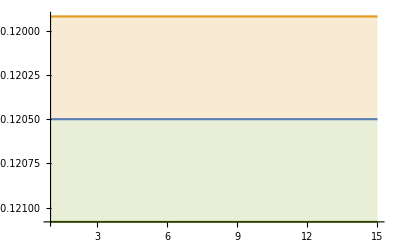

```mathematica
Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,15},Filling->{3->{1},2->{1}}]
```

```mathematica
SpoilHWFLOPlotN3=Show[Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,Length[meanErr2[[5]]]},Filling->{3->{1},2->{1}},PlotRange->{-.2,0}],ListPlot[{Table[{τSteps[[1,i]],meanErr2[[1,i]]},{i,1,Length[meanErr2[[1]]]}],Table[{τSteps[[2,i]],meanErr2[[2,i]]},{i,1,Length[meanErr2[[2]]]}],Table[{τSteps[[3,i]],meanErr2[[3,i]]},{i,1,Length[meanErr2[[3]]]}],Table[{τSteps[[4,i]],meanErr2[[4,i]]},{i,1,Length[meanErr2[[4]]]}],Table[{τSteps[[5,i]],meanErr2[[5,i]]},{i,1,Length[meanErr2[[5]]]}]},PlotRange->{-.03,-0.005},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]],markerlist[[4]],markerlist[[5]]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]},PlotStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau_{\\text{steps}}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3(\\text{NNLO})",Magnification->1.2]]
```

-Graphics-

#### QCD LO - gauss

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={430,430,430,430,430};
NWalkers=200;
Nf4α1LoopBig={0.21556,0.21556,0.21556,0.21556,0.21556};
aList={1,2,3,4,5};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
csvData=Table[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"],{xx,1,Length[aList]}]
```

({mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.01971468858875101, -0.02001743457984848, -0.020099952188832673, -0.019515137765829436, -0.020261531388952928, -0.020956241981041863, -0.02035912235046845, -0.019905666103554587, -0.020239953522197398, -0.019563086303087906, -0.019037163362446513, -0.01877146980789654, -0.018452943560142463, -0.01851127017167272, -0.018657625188978216, -0.01819841537200642, -0.0182735612599577, -0.018579974036589748, -0.01854064659016006, -0.01877920481426019, -0.019226367741686515, -0.019238465934231248, -0.019924852002075905, -0.019451773579784462, -0.01984600700190262, -0.019771097076641812, -0.020646048529079877, -0.02141153358234593, -0.01978059847058908, -0.01977681698334773, -0.019032176046117955, -0.01830911131319774, -0.01787083868432012, -0.017752953568705127, -0.017658274678899268, -0.017953112059142642, -0.018324438443798653, -0.018356410895552806, -0.01795977922821992, -0.017932447515213258, -0.017554270710280612, -0.01739444073911172, -0.017509052559106963, -0.017392595156385634, -0.01756683548423163, -0.017610397067840233, -0.017205693843563175, -0.016968232604419976, -0.01698969859320773, -0.016715631018714306, -0.01671124421572221, -0.016731107953680095, -0.017097328522091816, -0.01722405354158239, -0.01762091794952975, -0.01736516022826389, -0.01739505007382036, -0.01731058222294055, -0.017472748934582092, -0.017725079513256504, -0.01751869072235425, -0.017286643898274907, -0.017783567537983175, -0.017834076425415155, -0.017702332308448466, -0.017567118235199956, -0.017787508106362943, -0.01744083893140162, -0.018051660982915906, -0.018111235442215243, -0.018702719025080833, -0.01846631902691332, -0.018592578065374232, -0.018111964310036397, -0.018261566913543196, -0.018807679922322178, -0.019444036827722486, -0.018425790475916456, -0.020146445325032642, -0.02303212528545211, -0.021281586662776384, -0.019529903346374576, -0.020922411285521546, -0.019463532468753122, -0.02004920755596849, -0.02005943591081419, -0.020362497116889193, -0.019988577885829407, -0.01892577212111209, -0.01889796107436661, -0.0185905801505736, -0.018421419488329798, -0.01826729531445816, -0.01777574011400351, -0.017745086197182923, -0.017989968839609585, -0.01765694137427978, -0.0177848329458069, -0.01773557688823429, -0.017906990526180343, -0.017901361709679858, -0.018791361696520386, -0.018902411614191122, -0.018777308376084944, -0.01804390727996288, -0.018973566639833656, -0.019488496081732833, -0.0193674823301618, -0.020629249093158518, -0.020530186976383705, -0.020179642276351568, -0.01985633586680323, -0.019971857247372247, -0.019788681843772745, -0.020116077232065113, -0.01885868900065221, -0.019104326855693243, -0.017845901281610406, -0.018345484575967155, -0.019232568839124192, -0.01934031898686775, -0.01962922424956613, -0.019914915176873983, -0.019326312097842514, -0.01971512078945283, -0.019852395639012397, -0.020590570815265913, -0.01942075839200429, -0.019414844354681937, -0.019418158918755615, -0.019271331189346007, -0.019884405258031524, -0.019266708196235882, -0.01896226595165579, -0.019525777118919774, -0.019594263965127985, -0.019803885360283963, -0.01959723169407633, -0.019546930808611834, -0.019489920770523507, -0.01963271716617969, -0.01938182569670171, -0.023920096096803956, -0.025166585841131, -0.0196757514286188, -0.01979230638365864, -0.019641572000629746, -0.019396878741082067, -0.019235190446452003, -0.01923242399515701, -0.019146261168304004, -0.019191019800765652, -0.019292254714142542, -0.019341040087221203, -0.019567607342118216, -0.019847894541925815, -0.019630848423229333, -0.019282384460974765, -0.019283584460072698, -0.019798451465728964, -0.01977960594844721, -0.019910171493663108, -0.019831561445685632, -0.02015565181143773, -0.02107886522777203, -0.022549239914455448, -0.020619686971472987, -0.02007925435044898, -0.020750389397567782, -0.020917942692980297, -0.0209152621297911, -0.02256754976198619, -0.022751681206252233, -0.022524237941392303, -0.022461695436153496, -0.021933776135576424, -0.021390421100216137, -0.02093237554391831, -0.02162973974790559, -0.022360507466779835, -0.02094357041483927, -0.020890897009696617, -0.02171061879914318, -0.02328927905942309, -0.021972590768669167, -0.022479911186741048, -0.023778228037467247, -0.0212584656607151, -0.021001187079649535, -0.020945214216375938, -0.020607805928180623, -0.020786874950005082, -0.020605095248721818, -0.020734103535689198, -0.020497457765839087, -0.02045316830115634, -0.020204494394806517, -0.020597693846125555, -0.020053770246932178, -0.020515562589091187, -0.020204391166476036, -0.020464661613849466, -0.01985325720562199, -0.01982942567187306, -0.019757671158157773, -0.02047390860483247, -0.020428824447506294, -0.020395942790845233, -0.020556522841418113, -0.020583133693140566, -0.020492329564798333, -0.02077692508668623, -0.021154563654719256, -0.021593702985624123, -0.021608692308036297, -0.02183650708921964, -0.020673322547018955, -0.020990161095888846, -0.020291086094931927, -0.02017936924899893, -0.020439211219655053, -0.021199358851877362, -0.02046349946522531, -0.02087556771645068, -0.020994940078411583, -0.0200137539315617, -0.019884318253448403, -0.02024239676697435, -0.01986320189535528, -0.01989556610278838, -0.020122862414850444, -0.020205637128848018, -0.020130374873130845, -0.019822530026795602, -0.019964092943637515, -0.020740890653338513, -0.021623212334966346, -0.021325532699023125, -0.022915759713502785, -0.023217083848713193, -0.021467401162930735, -0.02208674983718013, -0.022125567918739573, -0.0216130078547119, -0.021691595411853584, -0.021066050439912266, -0.02115926903354588, -0.022320279967441223, -0.021694455874320336, -0.022182055820513247, -0.02133496550943241, -0.021829242309903126, -0.021418169454082925, -0.023285292244349068, -0.022451284601097563, -0.02198587441844623, -0.021245409482311357, -0.02044947012308274, -0.020384312904880658, -0.020428037155642082, -0.01963650459774765, -0.01908662237810539, -0.01989159438464696, -0.01947762174162689, -0.019559785888388626, -0.01991523879510095, -0.019218586429293832, -0.01903382428259275, -0.01892970184504037, -0.019619882788753058, -0.01962420525980539, -0.019619622644278755, -0.01947562698130532, -0.018681701558683365, -0.019128179327632302, -0.019266602713428883, -0.019099784267501623, -0.01969994606678798, -0.020067911363782383, -0.020147828921694283, -0.019716144022492284, -0.019244390480865327, -0.01923569030372207, -0.019565386322488106, -0.0197587470079177, -0.019265272785583914, -0.019813793302155477, -0.019895352561191335, -0.019718697136968596, -0.01950263295232452, -0.020101504435093818, -0.02119363433496162, -0.020561120487181332, -0.02135596248947478, -0.02128022785889768, -0.020956850057767006, -0.020611851836490953, -0.02106746700468825, -0.020566669303731036, -0.02044881564681373, -0.020667585301143633, -0.020898035496927484, -0.020629535662894195, -0.02102943281656528, -0.02087469426959366, -0.020934413188640068, -0.021161737839864442, -0.02152067960082559, -0.022157720409226592, -0.021776261179608982, -0.022270790219490647, -0.020678089498126297, -0.021621102453642425, -0.021408493648742147, -0.022112448007567523, -0.021044209294063324, -0.02153061910464577, -0.021192944335665733, -0.021232355050392428, -0.021094147572797744, -0.020776425930848913, -0.021202703606368875, -0.020502136023734602, -0.02073993609079539, -0.02045850893110427, -0.020339483440816333, -0.020648253023104694, -0.020410327449820527, -0.020483230833642497, -0.02049113754329991, -0.020810044385248083, -0.02094392078484752, -0.021224979520883775, -0.02196577341792898, -0.022607728206548532, -0.023949848484554618, -0.022069353604471372, -0.02282744961807682, -0.028889973580198236, -0.02350216324078209, -0.022390490989798967, -0.022570159132824348, -0.022424305317779964, -0.024523370557772973, -0.02298841764939894, -0.02283995881732832, -0.022147465862073605, -0.02249578484458347, -0.024533855246633374, -0.023867556881883606, -0.022894627487437747, -0.022809106324144485, -0.023599832943588344, -0.02453183778467712, -0.024078684384149916, -0.02308000188483252, -0.023530528063066797, -0.023069575514074875, -0.023193998488898082, -0.023389163821432614, -0.025087564789790535, -0.025034652309386674, -0.02435090728728374, -0.02689645910860974, -0.025026515448556406, -0.024795976351064945, -0.02449211518921321, -0.024441668971365495, -0.02559408649148284, -0.02443157656102399, -0.02454594983964606, -0.024911805002628205, -0.02541999056129104, -0.024627284026475158, -0.024155041877961896, -0.023617713280498918, -0.02360615307091305, -0.02431306769382419, -0.023995969292099618, -0.02404140351504154, -0.0246886549752986, -0.024586709140673867, -0.023924843555582085, -0.02367424856382766, -0.02465118868634607, -0.02465102728575417, -0.0239214713474976],[0.0014555004465598726, 0.0014502203861920095, 0.0014337188252655589, 0.001648632278881902, 0.0020571224994105357, 0.002422078913437176, 0.0018821023338252312, 0.001507988986741819, 0.0015778834140179677, 0.0013712992884818902, 0.0012012206028704123, 0.0012211890996757968, 0.0012030352782042323, 0.0010343623710347197, 0.0011798222503175979, 0.0009699004117000669, 0.000999467314833851, 0.0010616145660925476, 0.0010729851575942998, 0.0010826863577347147, 0.0014024842821816954, 0.0011859639316840228, 0.0013942150571308416, 0.001328549121070968, 0.0015378788004371416, 0.00174027784470684, 0.002657558033015092, 0.0033927876976955333, 0.002236884907507759, 0.0018996736247267195, 0.0012971370082027946, 0.000969605477531373, 0.0008951226616366617, 0.0008681376943613534, 0.0008630041026452959, 0.0009722114528086369, 0.0011171232626407215, 0.0013024052283891403, 0.00102701999333493, 0.0009571319409652635, 0.0008164164377006575, 0.0007636194584023842, 0.0007620069837863737, 0.000783464388130353, 0.0008273735913199738, 0.0009533459971974596, 0.0008174310740349356, 0.0007616960654963105, 0.0008240715979411224, 0.0007306899423635405, 0.0006767342894056856, 0.0006272218543239593, 0.0008429413723141688, 0.000952857599568249, 0.0013268753744899184, 0.000986701809862817, 0.0008694827084975725, 0.0008380257980968313, 0.0008350055832413016, 0.0008934234120448212, 0.0007633890814951486, 0.0007282027866570279, 0.0008761332606534723, 0.0009995153038577977, 0.0009596343296598824, 0.0008335792682342831, 0.0008600376582686466, 0.0008310359766787071, 0.0011151322367793188, 0.00106852822380169, 0.00122847379374503, 0.0010865062535314652, 0.0012229682215203247, 0.0009302141990640369, 0.0009632370677691118, 0.001318756510487568, 0.0019017653345211813, 0.0011723250797547522, 0.0027103067129199206, 0.005429138270980093, 0.0034138702741555076, 0.001689413868000056, 0.0035148869072686596, 0.001691747242672244, 0.0015957035574238345, 0.0016324989074559767, 0.001745537645594997, 0.0017510293108545338, 0.0012484507788334258, 0.0011601850227168464, 0.0009941416664814588, 0.0009391007949162802, 0.0008685494870188452, 0.0007635507571733043, 0.0007561469395628553, 0.0008359969712845489, 0.0007604041737329176, 0.0008581922980256177, 0.0008191815169964512, 0.0008712918879247872, 0.0010417713625875263, 0.0013802670652821056, 0.0012857083694987827, 0.0012236249112546839, 0.0009254553889871575, 0.001208555521049905, 0.0013183148396750577, 0.0012587511144470079, 0.0018893230689634396, 0.0017315671445116809, 0.0015454163257988339, 0.001289289417172577, 0.001341233462664829, 0.0013342432142510866, 0.0016079515991913216, 0.0011759173598291108, 0.0014848363227919874, 0.0008024156291758743, 0.0009558986912576248, 0.0010944049248407892, 0.0011636056317657199, 0.0014251508960243392, 0.001270187866680848, 0.0011083211210687002, 0.0011899059075363256, 0.0014735587386757744, 0.001837592756193309, 0.0010018734835146013, 0.0010273331396342441, 0.0009252910688809468, 0.0008754699776422434, 0.0010462021516092492, 0.0008030701547989656, 0.0007645655075733715, 0.0008736327391856717, 0.0009537312492580504, 0.0010180713046018996, 0.0009290711907651081, 0.001029027075753793, 0.0009793775484105037, 0.0011901402630602113, 0.001152244303197614, 0.005403933854288725, 0.0064292537374110075, 0.0011482630565243994, 0.0011132857498100657, 0.0009156331082845489, 0.000890800267327637, 0.000852182682787918, 0.0007796216418078423, 0.0007537529392385501, 0.000786067694240898, 0.0008338616145165282, 0.0007741029893320352, 0.0007996503454810126, 0.0009942470801264285, 0.0007974619327046948, 0.0007451257741739919, 0.0008036668203131606, 0.0009515632693410115, 0.0009567809538245784, 0.0009593611123367749, 0.0009236385688994284, 0.0012403466443746927, 0.001536728164747581, 0.00265207210971763, 0.0012608405243757577, 0.0009222197343078735, 0.001148163054845403, 0.0012492036209804567, 0.0013387370257364165, 0.0025057610745600886, 0.0028143762100984486, 0.002559169912410205, 0.002521722418743435, 0.0018371265652646102, 0.0013609505310042318, 0.00118025791781791, 0.0013570439005790402, 0.002305300690094349, 0.0011933210072681039, 0.0012490645102526904, 0.0018111068264651808, 0.003016024931344218, 0.0019452813757663665, 0.001781787740141016, 0.0026050317598744367, 0.001573940700891228, 0.00138027666466939, 0.0012863786220346568, 0.0013186155418818547, 0.0013337782881884712, 0.0011395937115355546, 0.0012186119988982515, 0.0009445864853173378, 0.0009462361774247526, 0.0009110131329123827, 0.0010086269718440953, 0.0009004554126297846, 0.00100921668439704, 0.0009294620425668274, 0.0009264872605462621, 0.0009065907419972119, 0.0009164101815916301, 0.0008859575519881829, 0.0011215572370494784, 0.0010560522201190341, 0.001013842846974743, 0.0011068819508704576, 0.0011475068252933243, 0.0010704358592518947, 0.001204685684173014, 0.001358427107235995, 0.0017936844573871614, 0.0016808542734987632, 0.0017017884537123646, 0.0013451043322521563, 0.0013287865665055868, 0.0011769958575458428, 0.0010515267148393532, 0.0011968119313210202, 0.0015036919177232667, 0.0011331832386313374, 0.0012757411241838634, 0.0012270618185656387, 0.0010055800194010488, 0.0009589638580312028, 0.0010004829379068202, 0.0009628696129489198, 0.0009456704978025156, 0.0010141079967477978, 0.0010881027140685888, 0.0010110701408254344, 0.0009917365634331688, 0.0010169231531820674, 0.001474014984918362, 0.0017594579605103927, 0.0013990335781339355, 0.002479719008462018, 0.0028434535748817357, 0.001446631954002313, 0.0019397877876277973, 0.0017132372484722333, 0.0015087127786134638, 0.0016952722537974787, 0.0015527653579600015, 0.001600736443974799, 0.0024275210729722205, 0.0015671698595956655, 0.0016696694586394052, 0.0014758163153612835, 0.0017186446498994935, 0.001562560931778591, 0.0021328419463500364, 0.0017901022500030304, 0.0016977884200105693, 0.0015425323846690172, 0.0013863470905505755, 0.0014349817112188135, 0.0013437103243230462, 0.0010879224444713413, 0.0009693685973357254, 0.0011360048744286067, 0.0009737461672437176, 0.001024546956622682, 0.0011579037896880635, 0.0010679139328109478, 0.0009867904357253874, 0.0009025051561574441, 0.001074561880464541, 0.0010461940118883376, 0.0010070061066494633, 0.0010196525193092458, 0.0009109237902092442, 0.0009994939860724277, 0.0009557753960109598, 0.0009451357057356627, 0.0011069907368736615, 0.0012375016849161884, 0.0011871920036985143, 0.0010212289977835378, 0.0009603490860920187, 0.0009538136155086056, 0.0010004603801284182, 0.0010109646523004234, 0.0008656690277116749, 0.0009988496684169464, 0.0009349784557380757, 0.0009017853539262133, 0.0009960395309573104, 0.001094784360356196, 0.001812687667181162, 0.0014611846505122384, 0.0019880353514806744, 0.0018547766653881318, 0.0013404844760454622, 0.0010821578634293903, 0.0014167518528534057, 0.0011931134198138321, 0.0011016659047367137, 0.0011482992739387376, 0.0014477438481696257, 0.0012194242236415293, 0.0012231616571688226, 0.001210963145927773, 0.001183481959684618, 0.0011662759766152728, 0.0013284722559767212, 0.0015219638425284347, 0.00140306539580538, 0.0018111455286487321, 0.0009797171942024611, 0.0016112064044724744, 0.0016111630256162369, 0.0017509907039940868, 0.0013494119018355748, 0.0014595258916579022, 0.0013069952999400446, 0.0012454138553297685, 0.0012111000638771738, 0.001042972535053483, 0.0011818176149861845, 0.0010125933473639876, 0.0012529589629059347, 0.0009992960411786974, 0.0009731681688048744, 0.000986476773244125, 0.0009513124654190042, 0.0009557549665580923, 0.0010014333156038251, 0.0009716847639945182, 0.0009335251583996617, 0.0010004478358306556, 0.0012318793155547752, 0.0013804622963143756, 0.0021316236502116974, 0.0013210765708347473, 0.0015763147851496938, 0.006613265148444811, 0.0018742048452687528, 0.001366985336076655, 0.001349880437735545, 0.001314826841991439, 0.002139908827028763, 0.0015974777948105157, 0.00139327141539795, 0.0012093338608811643, 0.001302459117107296, 0.001786793794845292, 0.0016635055069000313, 0.0013821374562925479, 0.0013324768529341892, 0.001713460066174457, 0.002195464574992151, 0.0015847718066640672, 0.0012496776026293369, 0.0013119704938594286, 0.0012593425347247988, 0.00134302564191571, 0.0015598548801849658, 0.002675128317977551, 0.0023493470270714635, 0.00204329368969206, 0.004165971531338332, 0.0025987726698972684, 0.0019454709427174594, 0.0018088012308492179, 0.0016428411124285779, 0.0028793821385151228, 0.0018070059238979436, 0.001988077535410496, 0.001969243836735671, 0.00226830272284802, 0.0019162878013159875, 0.0015830337693224388, 0.0014285420688898113, 0.001462753140792617, 0.001669839791927332, 0.0014921443327175193, 0.001558660549864813, 0.001997537552421979, 0.002234933784777929, 0.0018190371356634925, 0.0015126170462835813, 0.0019554101355969637, 0.0017412741068366093, 0.0016430478782121746],-0.0180931,0.000213564,0.459877}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.016670953654173874, -0.016523681626474565, -0.01685278086242558, -0.016355662793689746, -0.016471441266872902, -0.016778741641675542, -0.016418908068064765, -0.016266332232206217, -0.016326109132478284, -0.016378635592901262, -0.016611727988751428, -0.01660545030334411, -0.016341745048486737, -0.016431167499498404, -0.01630429905008236, -0.01631995719570121, -0.01630108664828097, -0.016189994068361167, -0.016113380177381547, -0.016153103298064835, -0.016290027688724368, -0.01643877527491562, -0.016479670187080832, -0.016448209915449187, -0.016202594267582204, -0.01630024417986414, -0.016367590303059665, -0.01620187887789871, -0.016204915364766388, -0.016238389015687336, -0.016207812025066968, -0.016289036323702877, -0.016257191550384503, -0.016340078656907085, -0.01635695308542549, -0.016198230281063097, -0.016342987560417983, -0.016280518813276534, -0.01624374797149982, -0.01635395690171287, -0.016154349883768647, -0.01612112939679511, -0.0161066025050067, -0.01613796839047893, -0.016206386986571338, -0.016224443896103304, -0.016201751466183918, -0.016216099124494773, -0.01625981981370772, -0.016074891155205714, -0.01605084589565284, -0.01596564834917119, -0.015821618388691984, -0.01600257474673976, -0.015946563291972242, -0.01573391024520666, -0.01554267015188265, -0.015503346748647336, -0.01556156861619923, -0.015581256677426585, -0.015674274479704615, -0.015576632491172112, -0.015612942557575456, -0.015546678365730041, -0.015555889728288292, -0.0156851551304821, -0.01593037429290684, -0.01600591893507063, -0.015883962290439705, -0.01577918989118583, -0.015827434123758585, -0.015901652997467916, -0.01584837706951028, -0.015766544592317414, -0.01573346819611118, -0.015795371928005942, -0.015897663331344083, -0.015939146303646068, -0.016014148527434872, -0.016109915976182908, -0.01605928715271865, -0.01603148826701084, -0.016001737995151758, -0.016075713237390918, -0.015899663120322396, -0.01588882275894642, -0.01598849760895418, -0.015902478107673125, -0.015879118564097672, -0.015986251026833185, -0.01594534380404792, -0.01600043304290042, -0.01618801481318075, -0.016121293978791137, -0.016006037041282128, -0.0160372096419574, -0.01604532959692104, -0.015933675463563033, -0.015859927826786777, -0.015817367985778607, -0.015631792479815696, -0.015600806452820451, -0.015587597862779606, -0.015480729280782564, -0.015566121442554237, -0.015617742389398481, -0.015574652697613543, -0.01560843009124411, -0.015599184809982763, -0.01569039341461431, -0.015727472972830007, -0.015608024295752403, -0.015633510712227735, -0.015588192724648797, -0.01562737891642166, -0.015656665502431687, -0.015652491584682026, -0.015687162441920307, -0.01564674515948211, -0.015849765522186674, -0.015818310609766566, -0.015875853342759375, -0.015767716612838753, -0.01579917392919309, -0.01569969891449388, -0.015787963217232005, -0.015858598873350463, -0.016038512744401247, -0.01605378887404777, -0.016127967347387934, -0.016255824769449444, -0.016267526509136418, -0.016262738451706178, -0.016425550894759514, -0.016617095851854755, -0.016702073283189168, -0.016810576142602014, -0.016937783992298554, -0.016805785588403267, -0.016841536223297076, -0.016634917265821905, -0.016509458224665846, -0.016355606248427572, -0.01632537727273958, -0.016250951378278613, -0.0162906149446832, -0.016190703116969487, -0.016213374619114148, -0.016102719619126706, -0.016044542387427436, -0.016032947267709586, -0.016008898129921404, -0.0160336356757582, -0.01605684708591692, -0.01614074382625952, -0.016081443566931412, -0.01639353959647944, -0.016587240702437576, -0.016371418104509955, -0.016450440005222538, -0.016592065343492664, -0.01670075591285529, -0.016827254942830622, -0.01710016603883457, -0.017485719233488323, -0.017907933532662162, -0.017549643260370496, -0.017508235466964818, -0.017563492961623194, -0.017861796584735724, -0.01814937875288898, -0.01725752236460284, -0.016993894540869477, -0.016823356847855287, -0.016631855575266478, -0.016730198107548572, -0.016554260328796016, -0.01654883147054845, -0.016513822391692225, -0.01655460318900892, -0.016709079330039928, -0.01642621440370894, -0.01648685827059922, -0.01643193264038427, -0.01656714623182365, -0.016805732688098884, -0.016963408397519274, -0.016991629698170252, -0.017253840608407733, -0.017441195377186483, -0.01703333576052526, -0.017026303266010803, -0.017243829293147977, -0.016988329669515325, -0.016993424509797614, -0.0170515628073903, -0.0168197269521078, -0.016651388543134745, -0.016672725916819522, -0.016972279310792617, -0.017198843456722394, -0.017008662992665288, -0.01691209921737734, -0.016903090034619817, -0.017018911394256597, -0.01731043937361824, -0.01772970269443061, -0.017656577510259765, -0.01760923628515204, -0.01730125298178941, -0.01755643689550296, -0.01778640315662073, -0.017515201673263127, -0.017479260896434333, -0.017968205212445, -0.01819490838319455, -0.018670579308464334, -0.018260631809314105, -0.018223350637963515, -0.01826798865646109, -0.018258474942212694, -0.019489158278927946, -0.02054617825665541, -0.019064565554895815, -0.01876294407997529, -0.018277936834545736, -0.018328475837076887, -0.017655958683164122, -0.017788765396707366, -0.017756155736443485, -0.017637598187948637, -0.017920224617901923, -0.017993511724369804, -0.01798579221899392, -0.018386908864853353, -0.01818590359999495, -0.01845159668570866, -0.018162356818861566, -0.018219712225677056, -0.0179646636121179, -0.01771947262268759, -0.017539675256678135, -0.017262350725993438, -0.01720221793891266, -0.017139008815100016, -0.017559067830765135, -0.01764343313704808, -0.01734052266109374, -0.017185451586989902, -0.017079270340595535, -0.01699562729560975, -0.017257759405577732, -0.017232055438353013, -0.017230768832091407, -0.017062666265541475, -0.01713351017046186, -0.01729528876286906, -0.01705987547646672, -0.01724559257285825, -0.017782647285639795, -0.017756586956430325, -0.01788620079277736, -0.017729760814853442, -0.01784352261520709, -0.017698207607886384, -0.01771775223306768, -0.01801226823413612, -0.01848515931333887, -0.018029548763573242, -0.01776322322595788, -0.018022513170563324, -0.017577921422170763, -0.017672507669035675, -0.017761975425002584, -0.01748775045674329, -0.01762018643728555, -0.017649698794781944, -0.01756799141273787, -0.017367934918670384, -0.017450380179292548, -0.017639706486166355, -0.017915123303575274, -0.0176251275889847, -0.017649193273111135, -0.017710488235244695, -0.017795978238368662, -0.017980592166055326, -0.017929637161519213, -0.01780003025256768, -0.01761160516358189, -0.01768315345850158, -0.017578275138767703, -0.017660952635855116, -0.017713880840516793, -0.017725077759370468, -0.017650186450441495, -0.017861866249533287, -0.01819809799346671, -0.01829780656984546, -0.01824101388266963, -0.01826773604585575, -0.018124433931869865, -0.018253050633869866, -0.018578276625062416, -0.018971262174813527, -0.01909714604744315, -0.01914511695531776, -0.01899406651734799, -0.019042905941200484, -0.019219520331013432, -0.019753591220134707, -0.020395606822868142, -0.02006955721515538, -0.019332532415157932, -0.019729902846771934, -0.01911449165313774, -0.01921214410956106, -0.0191662311976641, -0.01919611525042694, -0.019094667794890406, -0.01946108299205785, -0.01978405086001892, -0.019733253581016748, -0.020646159261726093, -0.01952978137692676, -0.019504592270088977, -0.01945053368008621, -0.019588004514892003, -0.019775866493612352, -0.02048669204881135, -0.02015255147724005, -0.019399295449342935, -0.019172173182983112, -0.019059654349729113, -0.019137692728810905, -0.019464617730743962, -0.019091415004417613, -0.02051679369090871, -0.02003482911794079, -0.01933067458417071, -0.018976454086197463, -0.019162814713793094, -0.01842463827880389, -0.018902797301125315, -0.018824996647590138, -0.018800107787213954, -0.018651093547091224, -0.01896089072764525, -0.018405646405768902, -0.01840074960894726, -0.018137336277582766, -0.01827066960237305, -0.018106300393612017, -0.01843422474775935, -0.01866591871759562, -0.018723986849256854, -0.0186797583176269, -0.01852365746769385, -0.01837647816587163, -0.018307999186733422, -0.018618036255465476, -0.01853812278616791, -0.018731896719761342, -0.01901815210977618, -0.01895946057173723, -0.01882693569453244, -0.0190337247667224, -0.01916133373819799, -0.019375253476741152, -0.01839551419055229, -0.018053511532906685, -0.01763765110265548, -0.01770907727674906, -0.01758916586919872, -0.017653599531630645, -0.017667951714145966, -0.017691614480611427, -0.017908677173570867, -0.017692860215544594, -0.017622818571909685, -0.017659565735194508, -0.017813344348069797, -0.017836232419127428, -0.017984318556738675, -0.017954672168438334, -0.018041254071805093, -0.01835234404167807],[0.0006918337678131532, 0.0006546807477413911, 0.0008659500829020184, 0.0006273535992117525, 0.0006144446513540718, 0.0007504008004213956, 0.0005996341715402987, 0.0005708588443540937, 0.0005833060572923284, 0.0006076408831077001, 0.0006603949760737066, 0.0006721726509261916, 0.0006133528367848547, 0.0006242524831385102, 0.0006230421286740399, 0.0006356560651146274, 0.0006365273629969951, 0.0005927563231667791, 0.0005882564184398857, 0.0005786537825497906, 0.0006527213449094676, 0.0006681135583402711, 0.0006489582170383111, 0.0006674116142656018, 0.0005945998041639373, 0.0006181080196937763, 0.0006014895965485037, 0.0005569657308506905, 0.000564634827750367, 0.0005769925572022985, 0.0005886586539765146, 0.0005956365857109911, 0.0005969256110913216, 0.0006241465735563283, 0.0006241189466811932, 0.0005881167970161055, 0.0007092526778399398, 0.0006611558449349512, 0.0006180697569198955, 0.0006353643319536842, 0.0005880548090968678, 0.0006032680054870772, 0.0005656693283643635, 0.0005988614781531167, 0.0005985014032192191, 0.0005930170184764313, 0.0006023530068384487, 0.000588316367412543, 0.0006310071012866914, 0.0006366529515353398, 0.0006037141273113229, 0.0005889612195598651, 0.0005776669778027686, 0.0006613531696041651, 0.0006253108773937186, 0.0005533596658625875, 0.0004938419844376308, 0.0004760673159245844, 0.00047804081428973644, 0.00048556887270835255, 0.0005112833325130119, 0.0004730620039700453, 0.0004922706648983866, 0.0004891571639113637, 0.0005008166482873675, 0.000525167812605002, 0.0005910854872125538, 0.0005952034344338514, 0.0005808526697084551, 0.0005307365968632116, 0.0005129458320793513, 0.0005319784840034841, 0.0005147930717482045, 0.0005035555099156923, 0.0005121395901291882, 0.0005168292840199964, 0.0005594889418035638, 0.0005431052211332882, 0.0006007254847643836, 0.0006113866305032501, 0.0005803726256522829, 0.0005958477059831426, 0.0006065437302932453, 0.0006263922501836562, 0.0005834559809337872, 0.0005871720639760849, 0.000597384269918423, 0.000566750757756964, 0.0005858149985075263, 0.0006040452170113919, 0.0005640290674424997, 0.0006050059285342449, 0.0006941214308728127, 0.0006621988022874238, 0.0006989058658333245, 0.0006979565845795938, 0.0007015151071309365, 0.0006528868206863416, 0.0006471842041131847, 0.0006391878916208723, 0.0005842180662187453, 0.0005660319517030605, 0.0005547743704046653, 0.0005083874715247794, 0.0005291398582390771, 0.0005516134379056285, 0.0005429048097740216, 0.0005511859425732263, 0.0005325028660516574, 0.0005586564481225522, 0.0005844736064732425, 0.0005424040455558124, 0.0005607386672383976, 0.0005512501914548611, 0.0005556793323082932, 0.0005784479460302282, 0.0005986929381644998, 0.0006027001070590459, 0.0005697970893857166, 0.0006026835965893709, 0.0005803504108785708, 0.0006030305477979705, 0.0005909881073563138, 0.0006483134007468728, 0.000589641509625144, 0.0006154791003311637, 0.0006266797208857387, 0.0006603709804677381, 0.0006664088483008412, 0.0006784967666373253, 0.000688410412720626, 0.0006713872836229714, 0.0006882505469200175, 0.0007193478034780075, 0.0007471229951429792, 0.0008024840045367296, 0.0008375041712710321, 0.0008452431993753752, 0.0008186453282438002, 0.0008269232115710041, 0.0007358513721908701, 0.0007050164455515295, 0.0006538508358663002, 0.0006504130244669808, 0.0006054674852545681, 0.0006134961651605488, 0.0005970473526851263, 0.0005861833231399095, 0.0005658963795587408, 0.0005607384785763747, 0.0005626679192766347, 0.0005916015184265804, 0.000595191906131775, 0.0005725354288756387, 0.0005685916883806061, 0.0005624446559681654, 0.0006260953116250835, 0.0006754054746831808, 0.0006358465661428323, 0.0006540948898104539, 0.0007115668171751107, 0.0007610877654241286, 0.0008308548671750103, 0.0009649015542103249, 0.0011740976862171433, 0.0015159443706044564, 0.001357446025725455, 0.0012505101893309192, 0.001303428668643651, 0.0015420562389706618, 0.0018405784554248812, 0.0010245963713151314, 0.0008680361894498145, 0.0008009861238185398, 0.0006724441464814886, 0.000732740480973499, 0.0007035401775353628, 0.000720290695676998, 0.000666520952347723, 0.0006781552040356322, 0.0007307014425707122, 0.0006356013546034608, 0.000679907728102187, 0.0006813020360530752, 0.0007256102508600633, 0.0007547202996727777, 0.0007969786757699008, 0.0008399942912336182, 0.0009258087177643497, 0.0009909022637228158, 0.000867255048887751, 0.0009045548404954963, 0.0011381745124965433, 0.0009166714371125715, 0.000896094758916785, 0.0008670182418934878, 0.0007974740558511893, 0.0007280332982696308, 0.0007224029651132817, 0.0008107999080934785, 0.0008841113989950741, 0.0007782565696109136, 0.0007437334909072075, 0.000736900756994988, 0.0007456382907585635, 0.0008239312832817525, 0.000996035781687766, 0.0010195380356127586, 0.0009663777619848864, 0.0008225809226530691, 0.0009152659076868343, 0.0009951934829435308, 0.0008612799230409782, 0.0008771653048475395, 0.0009767716707407845, 0.001037561071154396, 0.0012450765170062706, 0.0011031334424869243, 0.0011613915988563268, 0.0012026651732290428, 0.0012393197099754352, 0.002013353712324546, 0.0029400283262752394, 0.0016277447962364522, 0.0014582621159450113, 0.001107901299904915, 0.0012688560317546372, 0.0009812641519376137, 0.0009936191150705202, 0.0009889890800458226, 0.0009063780769767219, 0.0009949922540580234, 0.0009842130797699101, 0.0009857292520475504, 0.0011183652456187572, 0.0011213883041720624, 0.0013237616549872384, 0.0011764178378385539, 0.0011991755532871336, 0.0011410078093675128, 0.0010894061762135702, 0.0010018640857799852, 0.0008582709247847189, 0.0007997060990358132, 0.0008165781028602829, 0.0010666209240344276, 0.0010295247676239802, 0.0009007105443967156, 0.0008076590537014253, 0.000804899873276955, 0.0008416727238020534, 0.0009376871524720028, 0.0009209763597857338, 0.0009204585612196626, 0.0008134502186560761, 0.000848842506777151, 0.0009401993984722567, 0.0008264130323741857, 0.0009209081536903188, 0.0010745371982242603, 0.0010476690691373196, 0.0010469330981868667, 0.0010065194703187427, 0.0010626413739378727, 0.0010458358774853812, 0.0010511095309402169, 0.0011578189906939706, 0.0014188411057722281, 0.0012388013856261114, 0.0011174970742584295, 0.0012440076512703123, 0.0010078386571242114, 0.001026804342554256, 0.0010087920434479253, 0.0009203513032496398, 0.000953608719239987, 0.0009368748229708712, 0.0009220905915219033, 0.0008931161133091414, 0.0009326052072318985, 0.0010333455577073935, 0.0012202594242919258, 0.0009776072085110772, 0.0009943392997237984, 0.0010132733338978652, 0.00101126781659256, 0.0010623352189672816, 0.001026029198782421, 0.0009413154895826449, 0.0008670831212782925, 0.0008944031891724857, 0.0008807124767578689, 0.0009536797547119996, 0.0010211859561322155, 0.0009591875470144043, 0.0009236016752157136, 0.0010149669217540784, 0.0011628230845845218, 0.0012662384933430368, 0.0012028482113661642, 0.0012109514252626706, 0.0010088585796381125, 0.0009769500731422037, 0.0010602945851255307, 0.0013066144294291066, 0.0013522326925817754, 0.0014065546620471272, 0.0013026885330913876, 0.001358529339441065, 0.001328010706806556, 0.00167518358725376, 0.0019561119788301805, 0.0018374407894727962, 0.0014160616007646394, 0.0015626119103369102, 0.0012349009356509078, 0.001261603927118734, 0.0012316425431909796, 0.0012986306243376001, 0.0011792182514178554, 0.0013326539497083448, 0.0014531323072023495, 0.0014240087185199764, 0.0018737225965462653, 0.0013210944951221153, 0.0013094442407351147, 0.001353977546700266, 0.001484691094437878, 0.0014473012202599952, 0.0020281818095995276, 0.0018059433490237057, 0.0014127290005836643, 0.0012348298259899741, 0.001275201186105499, 0.0012982889613119425, 0.001549552375210883, 0.0012983380359903201, 0.0022909780757366014, 0.0019056894922583423, 0.001522554042966911, 0.001277178391292954, 0.0014405485602711713, 0.0010202601087916905, 0.0012450960281336892, 0.0012545931339102844, 0.001274094164549171, 0.0012567905137035604, 0.001502917469228703, 0.0011893452473102683, 0.0012726447462865751, 0.0009539447305519066, 0.001050761597634774, 0.0008930928264403678, 0.0009951527656319327, 0.00110060086212156, 0.0011083929869137308, 0.001040993098622699, 0.0010039404396898091, 0.0010067233464296005, 0.0010162248724689136, 0.0010982423609342052, 0.0010532600858907486, 0.0011125013540923272, 0.0012552343125869256, 0.0012633569416122738, 0.0012064465182709812, 0.001281238850757523, 0.0013378740938859495, 0.0017423304936466087, 0.0010995832614437622, 0.0008976799213406688, 0.0007970992582909805, 0.000775900635407507, 0.0007393683053954821, 0.000743555226524708, 0.0008321329963218595, 0.0008495414882679616, 0.0008897554869626153, 0.0008848072794545058, 0.0008955262375321929, 0.0008978173016880734, 0.0009122716834089792, 0.0009055488947903447, 0.0009160959615730338, 0.0008721681457729408, 0.0009281734525318881, 0.001054583400810642],-0.0148307,0.000224615,0.198134}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.011817018071456091, -0.011797097276119937, -0.011764062914453106, -0.01177163153374004, -0.011805483686695949, -0.01174015705088802, -0.011771909325507729, -0.011839276674901542, -0.011826467634480635, -0.011851320427969648, -0.011951041581944814, -0.01195695133398003, -0.011909807955959733, -0.011892419849364988, -0.011892328268322455, -0.011886949661273438, -0.011883036712800096, -0.011913259714892014, -0.011945476509167028, -0.01196241941320038, -0.011934700109847544, -0.0119574872869593, -0.011938871511101299, -0.01193159555361089, -0.011928438570017533, -0.01196026273230432, -0.011962088617707397, -0.011973084210077626, -0.012013675266560175, -0.012001641046472937, -0.012021472083229082, -0.011998169535178144, -0.01199093873420181, -0.011962663907335708, -0.012034074024974582, -0.012058154097631585, -0.012254304161392823, -0.012323143205156305, -0.012237198213789125, -0.012268137371505086, -0.012256512919072196, -0.012280663644850894, -0.01225768335697787, -0.012312103755375814, -0.012306154493298185, -0.0124118179108708, -0.012480757273800042, -0.012549014102213589, -0.012583412542664898, -0.012490762342975128, -0.01242335419163962, -0.012518299468482956, -0.012328754745516144, -0.012363074139210383, -0.012326327236881807, -0.012389836373237385, -0.012426048085941221, -0.012260814303695479, -0.012294945478789768, -0.012551470934244103, -0.012353134723541676, -0.012262149238122098, -0.012563982538884556, -0.01249206547946798, -0.01219656761295905, -0.012254257524203746, -0.012134988350565212, -0.01212693154863998, -0.012217648557089815, -0.012196439577638173, -0.012304075847877531, -0.012290756643321141, -0.01228712776319421, -0.0122685821483197, -0.012197171814276962, -0.01226325412207206, -0.012250707459076365, -0.01230471095112296, -0.012303867092755667, -0.012364497378599014, -0.012366450491445278, -0.012364341686207224, -0.012289940522265324, -0.012330472117049856, -0.012432704057793287, -0.012475813481992327, -0.012388329953401183, -0.012366934749198762, -0.012343499876010113, -0.012306971569332132, -0.012304601429291864, -0.012328550271909317, -0.012313207267682591, -0.012341330052344255, -0.012355698318704922, -0.012406655633535964, -0.012317475158997006, -0.012317882105929667, -0.012244519371165772, -0.012308020404172204, -0.012321542719228147, -0.01235312590512738, -0.012509521185988155, -0.012997485571838177, -0.013338954469113954, -0.013055574587979481, -0.012415384274224945, -0.012421224388092532, -0.01254450772800179, -0.012489552515215073, -0.012357704678904695, -0.012343538932576207, -0.012306818361526204, -0.012277698121277969, -0.01212511564255115, -0.012034724209274818, -0.012066735243910153, -0.011988800367297223, -0.012142679166231933, -0.012169462396772005, -0.012240200353110001, -0.012166438694562172, -0.01213116902382863, -0.012105815440938557, -0.012088283186202827, -0.012020168537236703, -0.01201056068309154, -0.012058534215655538, -0.0121243376778667, -0.012120481599253306, -0.012088730731899235, -0.01209126416397324, -0.012088289792740927, -0.012054824471368178, -0.012079430153579778, -0.01213334815009852, -0.012127797470032474, -0.012205348027970363, -0.01221549382629988, -0.012327532353207707, -0.012285385852660992, -0.012285224808809838, -0.012239698093470554, -0.012303250456036677, -0.012237043174237334, -0.012253494380907694, -0.012293929665493945, -0.012371516635975957, -0.0123768106492548, -0.01230959811312793, -0.012250184537751374, -0.012271716207902792, -0.012306905461603356, -0.01230843831481527, -0.012334770403399286, -0.012205806188832087, -0.012232211185408372, -0.012290531149167625, -0.012307678222818873, -0.012270264671496084, -0.012201884672376784, -0.01226904850883814, -0.012244956183132958, -0.012233729747143835, -0.012286036509103794, -0.012335258483354688, -0.012484317255316495, -0.012584147393038467, -0.01264620510499329, -0.012572620732815924, -0.01270386543559413, -0.012444509564435817, -0.012490414270472318, -0.012441263596711593, -0.012350593660574352, -0.012393473716588421, -0.01223867938484075, -0.01216919326409183, -0.012119912168149801, -0.012241055469031916, -0.012137210146639484, -0.012054979392424578, -0.012084292809087802, -0.012049364456616177, -0.01209490506267296, -0.012111045233941799, -0.012211012462433618, -0.012217390202595631, -0.012251276305876213, -0.012261563091944996, -0.012247256330147123, -0.012248705435373765, -0.012286347060224533, -0.01231490450393268, -0.012323299077082994, -0.012372161896575659, -0.012346743404486467, -0.012284272581014768, -0.012241303717981006, -0.012197191716388297, -0.012270773120833939, -0.012394079673415916, -0.01251763598609142, -0.012445344610683792, -0.012531640267830607, -0.012475343209413792, -0.012501532998962716, -0.01255418581749089, -0.01262515451494074, -0.012817667085637975, -0.012861481252883805, -0.013041290975700611, -0.01300836721510613, -0.012963277519201817, -0.013175670575422493, -0.013267080204837054, -0.01300193520375317, -0.01302577167500937, -0.013816881860289296, -0.012886744056546292, -0.012787760428863142, -0.012671655272060543, -0.012568299925249887, -0.012447418473749803, -0.012449604684633646, -0.012423315536204951, -0.012499701615225347, -0.012559799437410231, -0.012662161328465728, -0.012669921505403645, -0.01259630762875393, -0.012601918855011524, -0.012634229334045653, -0.01256714856516153, -0.012648681488605753, -0.012488728709312459, -0.01242795419738597, -0.012419497021035748, -0.012443289430722999, -0.012452319056179353, -0.012456138680586579, -0.012464583395881407, -0.012524148200159235, -0.012606017769936253, -0.01256146553191302, -0.01258951891449523, -0.012797823934205291, -0.012756727090459268, -0.012989015247647923, -0.012889832232901962, -0.0127420250252084, -0.012821268575364581, -0.012718688078973377, -0.01259684368946261, -0.013068290556081882, -0.013139304103951668, -0.013087511173841826, -0.013489168216089515, -0.013413800102503383, -0.013589076274773534, -0.013072478248170455, -0.01318713485639057, -0.013199856759296165, -0.013855134364468858, -0.013695377486632115, -0.012970945992214818, -0.01294602615136487, -0.012847254648981147, -0.012755080219318782, -0.012865164048002586, -0.012767354616167613, -0.012855767028881663, -0.013016769000090416, -0.012944613809119935, -0.012968600876733013, -0.01311326439395919, -0.01307476224951668, -0.012981714407075157, -0.013015881818185786, -0.013113800222860812, -0.012967939541596646, -0.012979619330388346, -0.013067302982436638, -0.013182802750311657, -0.01304641467672408, -0.013002151047114935, -0.013073392031968228, -0.013378929672647404, -0.013459335175593449, -0.013110500971385886, -0.013099960757417605, -0.01300866999146607, -0.013046914559728538, -0.013131016551813241, -0.013124432423536116, -0.013101873029220822, -0.013188576294871131, -0.013223021082818878, -0.013428926898396485, -0.013565009728036183, -0.013508004069478547, -0.013687969263686643, -0.013563439633027032, -0.013485680390207193, -0.01323381478285805, -0.013132895737598347, -0.013099753158729409, -0.013204505536015928, -0.013379566607066292, -0.013595886568723478, -0.013915306998267967, -0.013956300867090246, -0.0138035294276489, -0.013919438455936475, -0.013776667346626713, -0.013906326061063673, -0.013862461121733864, -0.014691256073287912, -0.014536211417765984, -0.014534107209307418, -0.014350972321690237, -0.014177004800847243, -0.014158978869971065, -0.0139598539490895, -0.01381902515863406, -0.013777635693558025, -0.01352743056803716, -0.013260074422602047, -0.01315152516676726, -0.013218517314232861, -0.013151653883317566, -0.013164188467276275, -0.013260899271881342, -0.013446347633746282, -0.013407726167745087, -0.013343198075462075, -0.013501306820681349, -0.01339052402590937, -0.013387681291391519, -0.013502476061723471, -0.013526186624100604, -0.013537572638602844, -0.013594869522257013, -0.013661053923166643, -0.013783256980923381, -0.013851964081383086, -0.01374569390488288, -0.014011881520163522, -0.013832611648930224, -0.014110974460841681, -0.014093666475130424, -0.013934388963028756, -0.014296540123871736, -0.014265348797527416, -0.01488595457018058, -0.014504135647546436, -0.014304578758104152, -0.014406847606598, -0.014404055796875792, -0.014577709941546292, -0.014566549571891654, -0.014642275055443082, -0.014237391006964266, -0.014512435039939575, -0.013996035963231035, -0.01432469714416588, -0.013997122894263029, -0.013795568998066887, -0.013720586225588555, -0.0137097278337507, -0.013748855542791953, -0.013725324274548898, -0.01354049820116365, -0.013547410247388673, -0.013726278663675168, -0.013634564620843096, -0.013621954927464841, -0.013616239617334993, -0.013689918157901299, -0.013568559613996565, -0.013591610083594819, -0.013574436581332875, -0.013473114347193841, -0.013373932013355114, -0.013314148935479046, -0.013303314239904865, -0.013372878280804391],[0.0003605188981198974, 0.0003571701574030005, 0.0003499422773748861, 0.0003487249046225463, 0.0003511350387419524, 0.0003397395043024568, 0.00034955267221555155, 0.00035912864925354736, 0.0003560453326426389, 0.000361894792485688, 0.00037521220595867783, 0.00037391248025187354, 0.0003725758212238739, 0.00037403373614085836, 0.00037220122961718655, 0.0003759062623996425, 0.0003688217798980266, 0.00037035724016708943, 0.0003745374849133258, 0.00037467250098892303, 0.00036830795234301983, 0.0003730102036595577, 0.0003666837295797196, 0.00036658386750495814, 0.0003671144823694937, 0.00036831807668808234, 0.00036398028814280234, 0.0003723880525915614, 0.0003770423862272112, 0.0003701166550505203, 0.0003813049037129762, 0.00037340096473267257, 0.0003677319941627119, 0.0003661065986550374, 0.00038272298506567, 0.0003868849557570472, 0.0004544751468180666, 0.0005094912528262847, 0.0004557961613922662, 0.00046051504493949293, 0.00046592610137579835, 0.0004768218086570453, 0.00048167711942668785, 0.0004977037585170049, 0.00047987353918348916, 0.0005159595324900268, 0.0005728192815575946, 0.0005754396816565037, 0.0006049146012507228, 0.0005393896800665156, 0.0005161693293117323, 0.0005567392709486259, 0.0004908644467581513, 0.0005206183951318599, 0.0004909774276800653, 0.0005445781726750031, 0.0005631858158942601, 0.000499248451054945, 0.0005252791869960827, 0.0008075555488570569, 0.0006380564073171246, 0.0005925140156013878, 0.000881266663479997, 0.0007983512179820947, 0.0005490164063838262, 0.0005556645427660625, 0.00044476278002613594, 0.0004380095517119924, 0.0004675258896580279, 0.00045155678893913227, 0.000484858296430814, 0.0004730860043377481, 0.0004494108980703213, 0.000467674769735389, 0.00044665575826978985, 0.00045636673955913365, 0.00044428644839133806, 0.00045140553557931353, 0.0004544956619695204, 0.00046382712438989524, 0.0004588868846701093, 0.0004631545791731362, 0.00045211320722880554, 0.00045948036419999954, 0.0004969046878774756, 0.0005122106566865406, 0.0004933639129925036, 0.0005019374120801154, 0.0004954124362211437, 0.00048219016753693047, 0.0004865471493934089, 0.0004980865215428915, 0.0004920425295587843, 0.0005090686576497116, 0.0005193892497566815, 0.0005250615778177317, 0.0005033068948467353, 0.0005154138433139232, 0.0004775307785511972, 0.0004931163540506537, 0.0005010554923233993, 0.0005317096166692674, 0.0006148881818259068, 0.0009170048661533597, 0.0013672929199817275, 0.0010509549084984668, 0.0005633071090147041, 0.0005581562007636022, 0.0006510924689718437, 0.0006072389338180286, 0.0005650079243220931, 0.0005209925427346867, 0.0005153788127777137, 0.0005069869927867436, 0.00047119996310390186, 0.00045778146914804456, 0.00047884958248651795, 0.00044121235546396487, 0.0004658181207948828, 0.00046811198096777354, 0.00048128688706521505, 0.0004537477583659142, 0.00044356972576357635, 0.00043687623596990957, 0.0004287724614267177, 0.0004161469704085596, 0.00040941599852404594, 0.00042223649897486163, 0.00043813418778345607, 0.0004441393579701614, 0.00043221302570887234, 0.00043008073441142507, 0.0004270606085106785, 0.0004170085020221734, 0.00042220588924590064, 0.0004360659563674894, 0.00043424062035738093, 0.00044774950467164383, 0.0004545391158702604, 0.000486690031718003, 0.0004607642936782073, 0.00046990063127996855, 0.00045218918117056876, 0.00047348474090313814, 0.00046108114811443636, 0.00046191432098272343, 0.00046820076466533013, 0.00048047371397359995, 0.0004879821999478592, 0.0004661270037414105, 0.00045382242124400625, 0.00045666604832730434, 0.0004670090756139452, 0.0004675934326469373, 0.00046280311165326885, 0.000436038202014176, 0.00044325283535770363, 0.0004599615803216378, 0.00047225525894906237, 0.000467584112249038, 0.0004566596709034645, 0.00048254759019036045, 0.0004812911325242053, 0.0004763380735424577, 0.0004942902119748579, 0.0005201553004872724, 0.000583773632664145, 0.0006369718814917065, 0.0007040174918568597, 0.0006750104957708364, 0.0007487774973997488, 0.0005883362922246818, 0.0006202251263891828, 0.0005983480250370976, 0.0005445824707598013, 0.0005810561681745162, 0.0005227822442699766, 0.00048334093210645676, 0.00045203731124408153, 0.0004809014395548453, 0.0004474670857261892, 0.0004277301249391892, 0.00043223414274724895, 0.00041928681882010585, 0.00043055017124776367, 0.0004299405306781551, 0.0004522819145928669, 0.000446634408817597, 0.000454763352573974, 0.00045067743773700915, 0.00044553749270519107, 0.0004490714916089649, 0.00046351537214810786, 0.0004670178819045602, 0.0004700787065843508, 0.0004982890959744051, 0.0004939418120719186, 0.0004828183406591098, 0.00047794443236030273, 0.00045888077328049703, 0.0004821406694785003, 0.000528963544531832, 0.0005547098536470463, 0.0005201177558666637, 0.0005559392889250566, 0.0005152503579630593, 0.0005291049098060435, 0.0005639555935053567, 0.0006231156343268532, 0.0007300408166711375, 0.0007529516867205029, 0.0008619009425662836, 0.0008654636102212801, 0.0008218001072566857, 0.0009946237892277706, 0.001190050066475186, 0.0009237769677440794, 0.0008902003184297733, 0.0016596226174593416, 0.0007874110962792441, 0.0007305611379702509, 0.0006444764265436449, 0.00061537679819143, 0.0005321060840712556, 0.0005385166860138916, 0.0005070153002433059, 0.0005203928561155431, 0.0005270776764205802, 0.0005634060006351002, 0.0005658405981704144, 0.0005324326130498568, 0.0005302027756425522, 0.0005256129270455446, 0.0005173204622145751, 0.0005500514696123001, 0.0005007176478486477, 0.0004934836289543143, 0.00048533869778682304, 0.0004853724182577976, 0.000489377094679438, 0.0004951696523955063, 0.000492637333659585, 0.0005100173320046432, 0.0005358860127543714, 0.0005223023176528927, 0.0005265595305548816, 0.0006159842834930331, 0.0006043890712986238, 0.0007257791745985639, 0.0006885253506755967, 0.0006371220970490709, 0.0006327377437251624, 0.0006133633618971912, 0.0005820370446431149, 0.0008367449594449422, 0.000882689307776579, 0.0008973481253472667, 0.0012667571129656322, 0.0011469114141750606, 0.0012397588927317111, 0.0008146956587454375, 0.0008190486112557841, 0.0008237634699645543, 0.0015164613829719532, 0.0013839097838635988, 0.0006602056159527639, 0.0006172980208828467, 0.000573354333759243, 0.0005721140163937816, 0.0005982866161462783, 0.0005425246284843931, 0.0005912478553402651, 0.0006849792503792366, 0.000648371658428557, 0.000676394524481671, 0.0007714848429954293, 0.0006780672376691784, 0.000618995075801384, 0.0006700549114645368, 0.0007543304726277813, 0.0006527005909438407, 0.0006558592573181267, 0.0006991434394499438, 0.0007897040623680305, 0.000727585203552349, 0.000698777925886085, 0.0007394276735345166, 0.0008902688305304165, 0.0009285309497737257, 0.0007092749359749619, 0.000678866505504183, 0.0006640512199215054, 0.0006876680707601498, 0.000731442485489157, 0.0007119890127934005, 0.0007190762316302842, 0.0007706093307420699, 0.000783122469659461, 0.0008978949658786774, 0.0009559497010175628, 0.0009129394002898232, 0.001046463976896792, 0.0009777148686235103, 0.0008911164047774692, 0.0007555666939006465, 0.0007035464516664724, 0.0007345269625097398, 0.0007661166248307318, 0.0007905532356313333, 0.0009730987662566467, 0.0012110607153762029, 0.0011836431373362455, 0.0010769607846891978, 0.0011058029844896074, 0.0009902955102912882, 0.0010403674460521715, 0.001048549773426482, 0.001585017157957693, 0.0015120075923553459, 0.0015425064416610269, 0.0014498883133836026, 0.0013350075122792416, 0.001222152738154757, 0.0010797751938075894, 0.001021516896685292, 0.001015979336711622, 0.0008655431156761888, 0.0007469609495711693, 0.0007274741242762004, 0.0007552671943885841, 0.0007404308300165937, 0.0007385187876171677, 0.0007698010370414671, 0.000811200626075243, 0.0008083795472934887, 0.0007626644628619774, 0.0007989506413022417, 0.0007740853011980933, 0.0007688102690512424, 0.0008332270925585472, 0.0008091183782645679, 0.0008494218168775322, 0.0008695675075167112, 0.0008915977085580052, 0.0009300088630560954, 0.0009887901828250704, 0.0009841307366414093, 0.001111248035736043, 0.0009548943451679787, 0.0011262353396703246, 0.0011244331565736945, 0.0011352497728199665, 0.0013853471695761017, 0.0014692440693380411, 0.002000205030726156, 0.0016158291319241164, 0.001438881423922999, 0.0014162687063034487, 0.0014198174865908844, 0.0014633539855945163, 0.0014453261015485853, 0.001520918049307419, 0.0012987290468461454, 0.0015179298178550145, 0.0012108856597898815, 0.0012936809640015294, 0.0011006522243122074, 0.0009810744750591164, 0.0009420270531822588, 0.0009324335443833167, 0.0009955557238190465, 0.0009852145251716146, 0.0008678047486088684, 0.0008932377513819422, 0.0009602033062362725, 0.0009559363926444864, 0.000887675146540811, 0.0009233602658643541, 0.0009670725031932456, 0.0008979304173391047, 0.000899228548509977, 0.0009066297060731072, 0.0008355878357353964, 0.0008168135322373602, 0.0008280101527561965, 0.000828201531451277, 0.0008862436950856354],-0.0108744,0.000189069,0.148083}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.009839527200454699, -0.009816236403090376, -0.00986101357377797, -0.010009489722091697, -0.010448934543182449, -0.010018074301361698, -0.01001395672878311, -0.009833192960043988, -0.00991382617372937, -0.009918704931907734, -0.009649270871183946, -0.009592628408227548, -0.009544771128774185, -0.009486298184390984, -0.00944174777541658, -0.009407280616451831, -0.009373613435218295, -0.009390807578039352, -0.00939673089206469, -0.009417977066323122, -0.009409330206446345, -0.009409252654851775, -0.009405400938309624, -0.009407126808840122, -0.009388080933214, -0.009414025988974641, -0.009407948793065621, -0.009425682379132865, -0.009397119364387098, -0.00936455580076955, -0.00937991914151552, -0.009372843941985311, -0.009343047661303127, -0.009342056533792234, -0.00936007729570926, -0.009368878776532199, -0.009401017921946324, -0.009401367928799408, -0.009388558391424915, -0.009418386215237688, -0.009438239938067495, -0.009411958688718679, -0.00940753491553389, -0.00942596742734603, -0.009483584679049266, -0.009531149051117325, -0.009528608239264387, -0.009617872936713135, -0.009567138514518595, -0.00954603135870219, -0.009502535829046402, -0.009543063314259494, -0.009474351203524743, -0.009501679383323185, -0.009520599023841341, -0.009472606473263636, -0.00946376474894548, -0.009473313818788914, -0.00950937969491301, -0.009547422333527124, -0.009590923013814543, -0.00958549358310275, -0.009569478713012237, -0.009616879444701219, -0.009624420770819089, -0.009587033286214793, -0.009608353939684126, -0.009666073210341611, -0.00966514094604598, -0.009630325667355619, -0.009710614447655414, -0.009701587697480753, -0.009659854703486103, -0.009678552937715678, -0.009655526570396328, -0.009628651533801989, -0.009628385343899554, -0.0096426950190247, -0.009616067016783624, -0.00960282750017263, -0.009545478535337762, -0.009504357473157404, -0.009481668217333204, -0.009483179005698084, -0.009514106879256032, -0.009553147378140343, -0.009606082084382822, -0.009624690327181051, -0.009689277904584835, -0.009716445167989769, -0.009797111330286495, -0.009813039095684878, -0.009896490743486407, -0.009856226576581518, -0.009836324140239253, -0.00980537828352106, -0.009822715084685857, -0.009893521476644405, -0.00988577224680174, -0.009896669338446745, -0.009901447301136559, -0.009947428824444477, -0.009986202007147144, -0.009855890198900447, -0.010205587017332738, -0.010047219837468946, -0.010012926203649073, -0.01009368831467458, -0.010015994117896365, -0.009963842624951005, -0.009970306595563742, -0.009940659791720033, -0.010019150226655098, -0.010051341528627628, -0.010085626463295218, -0.01011089960273069, -0.010114537248328581, -0.010199362219728718, -0.010329384221811113, -0.01035809901505864, -0.010366170215787873, -0.01129129698127128, -0.010578925444049758, -0.010321250644642923, -0.010252928037895596, -0.010341272501501908, -0.010495330312793072, -0.010603994882758153, -0.01064683692438853, -0.010594392025438772, -0.010285779242305036, -0.010086224825272324, -0.010068550413590205, -0.010016046461668262, -0.010061754051337612, -0.010077359506366384, -0.010086542366971221, -0.010064798938305317, -0.010013157181835557, -0.010036759172965887, -0.010093943456746525, -0.009977729939325225, -0.009934132471982143, -0.00998252039464612, -0.00997533363921843, -0.009931301493923541, -0.009953307727355901, -0.00989383100435171, -0.00989279323233762, -0.00987567585567535, -0.009889228313368643, -0.009943717387963201, -0.009926328815029379, -0.00994341935150876, -0.00990815479089179, -0.009913645159128348, -0.009925109753472059, -0.009934923899000178, -0.00993905679923418, -0.009921854063394804, -0.009900068494815025, -0.009886082760383505, -0.009964030970359397, -0.009908758700635251, -0.009906000030885523, -0.009954235437937409, -0.010063859847146504, -0.010114557186556681, -0.01009638258964761, -0.01007915244772559, -0.010105766160010975, -0.010178375337649306, -0.010092749622843197, -0.010158026048583119, -0.010332106487514123, -0.010274258808818203, -0.01060236494071681, -0.010497613365993875, -0.010589542728862932, -0.010466862343681193, -0.010265135943772583, -0.010192044383407475, -0.010143477949754155, -0.01029630218170394, -0.010347136704467892, -0.010364503867947896, -0.010484627200162099, -0.010480389968403251, -0.010417816441333314, -0.01054797663462903, -0.010557168164088736, -0.01042535299078822, -0.010366948354695277, -0.010316548940752669, -0.010290735666174415, -0.010221334556649347, -0.010161810790756894, -0.010195566321170758, -0.010118788986469781, -0.010156473577097742, -0.010106884839300358, -0.010025102123388491, -0.010102765997552533, -0.010149692039141662, -0.01020775659724572, -0.010377813864767825, -0.01040675722701855, -0.010462519162530371, -0.010441986897862281, -0.010372595195093665, -0.010374913688798115, -0.010431709672681182, -0.010484823494909833, -0.01050339545144271, -0.010560164917437774, -0.010341407193017514, -0.010260527843394577, -0.010356968797303636, -0.010260376171667121, -0.010302519066785159, -0.01028102165992289, -0.010274711985792846, -0.010233889340106609, -0.01024362872633749, -0.010322594843805124, -0.010252851843502579, -0.010267599598244465, -0.01024037227747734, -0.010223610074400525, -0.010374870507132369, -0.010396614859255403, -0.01029547363222254, -0.010281666167872745, -0.010264317642276102, -0.010288402080360283, -0.010327013870330533, -0.010304755296751808, -0.010302115521452866, -0.010312233727193088, -0.010313749833554892, -0.010404074216655542, -0.01052574119545052, -0.010507277641226042, -0.010507742157613801, -0.010508577302084288, -0.010408437134025065, -0.010362216918965281, -0.010415803833023715, -0.010429881590817067, -0.01042458391599224, -0.010455438391196618, -0.010349800918664002, -0.010350678700204372, -0.010333831817834366, -0.01034626393734224, -0.01024104902583678, -0.010223882138541328, -0.010262210206784313, -0.010247056600378824, -0.01024634136473403, -0.0102810194664897, -0.010264477218885267, -0.010260282799015162, -0.010234556950733862, -0.010187568650206424, -0.010235868925528132, -0.010236032613898792, -0.010119014707664348, -0.010093575098662773, -0.010111881767007681, -0.010071618466399162, -0.010141890135923298, -0.010172587806466474, -0.010081523155446756, -0.010087742479019403, -0.010072347807496645, -0.01004049489159645, -0.010070012090676636, -0.010120639221243722, -0.010092499408793438, -0.010117920819123986, -0.01015681497993341, -0.010197711407513679, -0.010188047253585861, -0.010187687166129326, -0.010242473131887154, -0.010235164504776278, -0.01023346965718478, -0.01028431322211913, -0.010326225890091743, -0.010285448372078466, -0.010250163920889089, -0.010189080235178982, -0.010185885289652854, -0.010235601554850586, -0.010318409467230156, -0.010249063733325178, -0.010233483755216315, -0.010199260480358772, -0.010174197877232984, -0.01020571344854937, -0.010345763650703492, -0.01030917336344731, -0.010300048611474608, -0.01032386508832451, -0.010333338765190674, -0.01032324351792581, -0.010294078712637737, -0.010306759375916942, -0.010170176050256835, -0.010188105931300909, -0.01012695817326313, -0.010104544529605138, -0.010158521763438608, -0.010135265533330058, -0.010100879002667925, -0.010195977454100483, -0.010237123335476609, -0.010203106823560648, -0.01015652288344673, -0.01009371785379391, -0.010177304016967956, -0.010209433707469797, -0.010242933150631297, -0.0102842982693236, -0.010310152429289504, -0.010334321267595023, -0.0102698397261629, -0.010273261889920546, -0.010302501071089674, -0.01040219965110325, -0.010448328408977636, -0.01051750187403745, -0.010423135401905873, -0.010551035802346268, -0.010681388411059672, -0.01076265546505689, -0.010892983685794265, -0.010966593089890833, -0.010669609466521205, -0.010702083947831044, -0.010761391305821134, -0.01069185998125881, -0.010527259937325588, -0.010550384805005312, -0.010459148771590092, -0.010425352037735185, -0.010412343565725691, -0.010475881341303717, -0.010563320311380778, -0.010591990397534869, -0.010689518558358542, -0.010798256790265881, -0.010922768880888733, -0.010833242948646227, -0.01083587465160109, -0.010808327595827385, -0.010784442122949775, -0.010755552343323182, -0.010785431216730777, -0.010712102329330458, -0.010735259822432213, -0.010684551047244558, -0.0108328313850901, -0.010824827914653933, -0.010908959545277212, -0.01086169146892589, -0.010965402503024337, -0.011044563790551675, -0.011130929191700799, -0.011287991141316822, -0.01127047590618767, -0.01104834415215274, -0.011175554187762587, -0.011004665936552454, -0.011099038066217147, -0.01107574898040778, -0.011033584577685511, -0.010885054774174173, -0.010818322867090282, -0.010810982251363743, -0.010755632917338965, -0.01074421009544179, -0.010687455379728707, -0.010777573808155068, -0.010712674730250482, -0.010706696696189849],[0.0006246961232611697, 0.0006126321588893742, 0.0006764713878685458, 0.000790123274100691, 0.0011693324613059183, 0.0008097630498191342, 0.0008055454815001904, 0.0006554086434942588, 0.0007250445792713811, 0.000722598254060754, 0.0004905520730443068, 0.0004493740519488356, 0.0004110174080920576, 0.00036681068662087183, 0.0003320014797275659, 0.0003207154569602918, 0.00030579168539052133, 0.0003059180294303523, 0.000305453806687595, 0.000313899445992009, 0.00030410414489237124, 0.00029862855178754556, 0.000301836616315319, 0.00030341676177254786, 0.00030150841045272435, 0.0003084582033720133, 0.0003056707111037847, 0.00031408772326833466, 0.00029943621683116705, 0.00029534181587446637, 0.0002950252543353168, 0.0002952576628265737, 0.00028925139243913785, 0.00028700490604346, 0.0002922366378249478, 0.000298920637507759, 0.0003150396692853425, 0.0003175820620201079, 0.00031755563888256205, 0.00032767952735453254, 0.00033291084359148194, 0.0003265380553725291, 0.00032447319301635375, 0.00033494679411020915, 0.0003547026187991253, 0.0003598471564999508, 0.00035712694387149543, 0.00038040047841486705, 0.0003640686060584472, 0.0003605481799676813, 0.00034081270967084457, 0.0003554873037363558, 0.0003439663914542562, 0.00035052240078744265, 0.00034365299718664143, 0.000334891442459063, 0.00033104231238487375, 0.0003350234119495435, 0.0003484965570466097, 0.00036021670175753214, 0.0003756041030775089, 0.00037687489932301495, 0.00037234288076046115, 0.0004107229305600397, 0.0004120169045233928, 0.00037824707531133975, 0.00037729872947706396, 0.00040666483955085873, 0.00040654177516264567, 0.0003902152269545325, 0.00041193752312823883, 0.00041443400247155175, 0.0003876669811745223, 0.0004134630785402601, 0.00040256024126667645, 0.00040144320644703896, 0.00040980973497448207, 0.000412267146880709, 0.00041189461734273346, 0.0003936391819738132, 0.000354657071727106, 0.00034114804780425236, 0.00033978111886413603, 0.0003382211024766431, 0.00034785060582135193, 0.0003619787967197224, 0.0003755124765714085, 0.0003816643149334793, 0.0004072481554920643, 0.0004177034496159153, 0.00044610523906601305, 0.00045763822058573936, 0.0004907852731004295, 0.00047244308392434335, 0.00046351589958159813, 0.00045370179342938625, 0.0004523894601212103, 0.0004877850165338404, 0.00048614033264728713, 0.0004940319221226315, 0.0005048611783308172, 0.00054279643220675, 0.0005693414991912706, 0.0004899127921676788, 0.0007354989337822059, 0.000594060029458314, 0.0005601681764175131, 0.0005932563000409439, 0.0005430029874450883, 0.0005299688725644561, 0.0005439829937295052, 0.0005268556534217162, 0.0005700415366248505, 0.0005632519237016298, 0.0005676004015930255, 0.0005865942093363745, 0.000591561718143068, 0.0006484938080361186, 0.000762193031922917, 0.0007511424415992443, 0.000767984294993655, 0.0015740362879445263, 0.0009504161934476687, 0.0007420626286268325, 0.0006628904932414222, 0.0007590085207056206, 0.000902826184949089, 0.0009889728209686367, 0.0010077503410549596, 0.0009657241567716764, 0.0007075055001295982, 0.0005559456764863559, 0.0005279627589477038, 0.0004933608609934529, 0.0005138032956247706, 0.0005249783826705355, 0.00051553732817773, 0.000500880120587378, 0.00047493691912824635, 0.0004743633309561915, 0.0004965275669663766, 0.0004695299361415093, 0.0004546648442695158, 0.00047306236813911767, 0.0004747796271270652, 0.00044414029371210855, 0.000465001882701916, 0.00042522130631273796, 0.0004311490997988309, 0.0004248420499177491, 0.00043060814834092203, 0.00046373270763013457, 0.00046111039056587785, 0.0004893873788717565, 0.0004676468681139193, 0.0004775082478376285, 0.00045502722580776446, 0.00046047917954495347, 0.00046794874703216577, 0.0004873657115914048, 0.00048029248893803134, 0.0004749866151979836, 0.0005292094826335355, 0.0004801159497089354, 0.0004654304946678014, 0.0004771109835125595, 0.0005347856116596536, 0.000543074321240679, 0.0005467071902108302, 0.0005391783814579258, 0.000565897993302097, 0.0006309599938297682, 0.0005869989013325784, 0.0006058452817024596, 0.0007134373361187128, 0.0007008168659533897, 0.0009793654438904264, 0.000899042537625506, 0.0009509121076140732, 0.0008623617217270368, 0.0006807503230241962, 0.0006438725278886106, 0.0005811825443731795, 0.0006743659185160755, 0.0006997756611373117, 0.000686483645215423, 0.0007466179709445061, 0.0007372403058310107, 0.0006459854561005258, 0.0007333209174400083, 0.0007624755411894694, 0.0006603392863783549, 0.0006204219973700492, 0.0006100418113040403, 0.0005844320128370787, 0.0005531543067277121, 0.0005318308841969466, 0.0005448902429734742, 0.0005058992950551387, 0.0005245149903345175, 0.0005048338946305002, 0.00047477087481617334, 0.0004963769896996494, 0.0005135622402102533, 0.000538538494057953, 0.0006280923942463994, 0.0006356408163765631, 0.0006506520526407478, 0.0006269806895399356, 0.0005913443038996224, 0.0005788609007081356, 0.0005983359828934214, 0.0006384457713817603, 0.0006369332866298169, 0.0006726971746074005, 0.0005529510698819325, 0.0005126493145868527, 0.0005495153583857747, 0.0005045707974931025, 0.0005318690587668313, 0.0005288274860286637, 0.0005245055612348175, 0.0005006582189502977, 0.0004932119167620039, 0.000521469315019391, 0.0004971803814356792, 0.0004922153921637382, 0.0004826619891832165, 0.00046563643021928556, 0.0005046378197511478, 0.000502883226734232, 0.00046123227738572073, 0.0004496215017834939, 0.0004481506366323719, 0.0004436263056105496, 0.0004562176898727839, 0.00046239637709862447, 0.000475511995051514, 0.0004792245579336432, 0.0004759099109996118, 0.0005118970298601805, 0.0005683398741148413, 0.0005438674118716325, 0.0005538634116945232, 0.0005568667132729158, 0.0005194450950826205, 0.0004958653781677106, 0.0005029702665898942, 0.0004904053529756597, 0.0004936825896185817, 0.0005070011594668673, 0.00046343149999007694, 0.00047652857605528723, 0.0004894239038801145, 0.0004884312376607742, 0.00045030308303246213, 0.00044771311812563213, 0.00045975124491571314, 0.0004577690949517622, 0.0004675138565390699, 0.0004869613671243112, 0.0004923470375877173, 0.0004950439062834736, 0.0004971891122379756, 0.0004546735474779918, 0.0004695937814496566, 0.00048368358180733326, 0.0004308973745522194, 0.0004298063148728027, 0.0004356070186885153, 0.00042734768155552123, 0.0004489792930933716, 0.00045697133945375815, 0.00042768644065944327, 0.00042677555039177014, 0.0004281817841244809, 0.00041109158291061044, 0.00042028613420966223, 0.0004456085486908377, 0.0004263704722909707, 0.00043821373500080047, 0.00045894421530398967, 0.0004908058412113136, 0.00047675053253712357, 0.0004694141137486794, 0.0004827213652833131, 0.0004854478107179355, 0.0004723466105679089, 0.0004687517989866308, 0.0004808838919466137, 0.00048062510303269234, 0.00046965365768747886, 0.0004535676582652896, 0.00044911213324516126, 0.00047051480535112704, 0.0005065909829611382, 0.0004871027820387747, 0.0004865326352915153, 0.0004796531312990638, 0.0004580512777322001, 0.0004648027692710306, 0.0005401611763692953, 0.0005281024337528605, 0.000501157909249664, 0.0005284043338002573, 0.000535559964149445, 0.0005246780667959869, 0.0005162575341101544, 0.000513028144297278, 0.0004563696193248972, 0.0004630040399945521, 0.0004277096147252544, 0.00043225797545208084, 0.0004674518697554497, 0.00045744765255179324, 0.0004373873023585073, 0.000484324667024271, 0.0004945511478123891, 0.00047960047063159674, 0.0004796671120473848, 0.00043424846025896086, 0.00047947038649289527, 0.0004797365000502828, 0.000500482006883846, 0.0005022325965752449, 0.0005041142396385802, 0.0005114959120880311, 0.0004814312483328241, 0.00048498837313386116, 0.0004835128002637502, 0.0005604254212619618, 0.0005979192407303765, 0.0006163793125054647, 0.0005414738522919265, 0.0005903536641628832, 0.0006475014055342376, 0.0006992210374996352, 0.0008249226426854303, 0.0008529665320717759, 0.0006274947893969202, 0.0006270244941749326, 0.0006729167825291135, 0.0006392008566672845, 0.0005360630735225049, 0.0005389652124472506, 0.000494479621201949, 0.00048456763566789976, 0.0004860236327469942, 0.0005008855722741963, 0.000526571774840285, 0.000527627396963872, 0.000560066425593583, 0.0006006929587363162, 0.0006430637512548523, 0.0006004220229088124, 0.0006078560184267296, 0.000607307563870039, 0.0005743144627180698, 0.000549831103921354, 0.0005820196689060284, 0.0005421735550918782, 0.0005703694655964318, 0.0005410920019143731, 0.0005959880773876632, 0.0006105262972716514, 0.0006474293343788225, 0.000610911306801719, 0.000639660609409875, 0.000698692168588311, 0.0007242743111339492, 0.0008208591248762862, 0.0008477499558104482, 0.0006655934476463058, 0.0007594098715829934, 0.0006755429915473274, 0.0007157711142815907, 0.0006642924094602097, 0.0007061330320490877, 0.0006269061266264168, 0.0005911648032065502, 0.0005669027509206486, 0.0005436250513405884, 0.0005332329531749111, 0.0005181568450970351, 0.0005478911586114139, 0.0005493469142209678, 0.0005368131686792438],-0.00897511,0.000176725,0.0882805}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.007925871681715218, -0.007970372980578006, -0.007986278861007131, -0.008004863037801992, -0.008016485899503378, -0.007986110575366067, -0.008013482635409552, -0.008011372121392813, -0.007999683973910075, -0.008066354262656809, -0.008031043488573253, -0.0080002382786797, -0.007973681210804922, -0.007970298597805644, -0.007972476326002736, -0.007969766262867132, -0.007944038351513099, -0.007939914917360529, -0.00795793665020592, -0.007940115058892657, -0.007914060476678027, -0.007892505363899141, -0.00790251215894649, -0.007939012244689646, -0.007924851217198043, -0.007936558990823805, -0.007951229917669585, -0.007963814550590578, -0.007933637417928028, -0.007932453020550732, -0.0079396730857761, -0.007955807474217013, -0.007930310949383356, -0.007909194699415702, -0.007901945335652567, -0.007903531122057033, -0.007901179469323323, -0.007909289113565287, -0.007923070616035616, -0.007921111557903097, -0.007943249354796032, -0.007959344642408366, -0.007955705903427666, -0.007923371435343125, -0.007931257700600595, -0.00797819800929826, -0.007963081617624431, -0.00800175465812489, -0.007962446267059426, -0.007965174536821867, -0.007943800691218141, -0.007928345529380704, -0.007900803232549977, -0.007894934498656291, -0.007910136890040251, -0.007886936048172961, -0.007873197888565458, -0.007844253986536076, -0.00782499085307611, -0.007816085174635556, -0.007822349259376306, -0.007838323053079119, -0.007805455569810196, -0.007826093169090513, -0.007864673060236875, -0.00785118194705521, -0.007871360686884819, -0.007874986139973497, -0.007870768646140246, -0.007881537240667397, -0.007881590043407414, -0.00786771683242692, -0.007869264224113152, -0.007852548985097574, -0.007858700751431292, -0.007878381511772057, -0.007868460686434467, -0.007876808199121847, -0.00787754344925275, -0.00790038121095037, -0.0078865517894066, -0.007882499730507314, -0.007876047718886779, -0.007891862760299052, -0.007907725458211173, -0.007909411611066097, -0.007918366565661777, -0.007929934634032956, -0.007934426283255724, -0.007949333712251422, -0.007963765491811452, -0.007959180407976505, -0.007956615674501446, -0.00793865412338792, -0.007939156724783661, -0.007924481276013811, -0.007926163248496196, -0.007953271093519199, -0.007991364026501671, -0.008021024135296083, -0.008107783877666419, -0.008090394501491792, -0.008087707725873592, -0.008080936962761121, -0.008179911915482087, -0.008187390389463471, -0.008149898533419556, -0.008083232679867606, -0.008056858885862687, -0.008109683068854715, -0.008111474318846611, -0.008128802405811158, -0.00813687658702774, -0.008124447117322988, -0.008192450359860265, -0.008122042743219288, -0.008102629342868749, -0.008112225594283788, -0.008078589998558016, -0.008083724844186947, -0.008111388948625141, -0.008130122421438343, -0.00816958986367304, -0.008158350125992666, -0.008157457681488327, -0.008165679361762938, -0.008303147350018776, -0.008337974522653531, -0.008327732593925873, -0.008225121114510339, -0.008135168942997125, -0.008168171200175824, -0.008174095503010716, -0.008121464073541224, -0.008111571185915854, -0.008100358722828086, -0.008102040039008695, -0.00810103592391716, -0.008070009906970984, -0.00807934351978236, -0.008098266697865971, -0.008079687578072687, -0.008067799613213451, -0.008059719204124254, -0.008054534083065671, -0.008028030767042268, -0.008046957923762565, -0.008036143393392509, -0.008043468790529012, -0.008077875758086762, -0.008074891711710235, -0.008085771493717796, -0.00807115489477108, -0.008119854775991794, -0.00814964126556745, -0.008122552551726336, -0.008131406230965445, -0.008161631916783301, -0.008153654881322466, -0.008121638651609288, -0.008135788211870793, -0.008096650613068346, -0.00809795649975048, -0.008084143683771002, -0.008085575232326355, -0.00808142666216839, -0.00813576671439489, -0.0081296334532695, -0.008116904655486474, -0.008098547610647048, -0.008171643324663752, -0.008218897382408805, -0.008163312876604696, -0.008180141691684706, -0.00830787735439876, -0.008368704990089126, -0.008229468816216516, -0.008083553322494384, -0.008136430799008899, -0.008142086295174834, -0.008081262892482285, -0.008045178554135087, -0.008078322307747, -0.008172241339665475, -0.00817553575604949, -0.008220478322672718, -0.00819385014072928, -0.008230114095524838, -0.008212452924408146, -0.008268328744139502, -0.008312894951931347, -0.008266450213573329, -0.008318602942645009, -0.008277874772708426, -0.00826269787029062, -0.008251419819110015, -0.008290844240186173, -0.008280319112411045, -0.00824750188001581, -0.008274056530043358, -0.008357343048330567, -0.008376700233401951, -0.00849474177472686, -0.008519229809979836, -0.008483492855656782, -0.008549231442871983, -0.008537356193930657, -0.008522961677633554, -0.008455864984720556, -0.008428686567187543, -0.008470423327097394, -0.008489847235101959, -0.008453735167922192, -0.00847589482582889, -0.008335399940256102, -0.008269792809148179, -0.008334855892168648, -0.008505438468895897, -0.008434994627746505, -0.008618118672212254, -0.008823843307149592, -0.00887819690187845, -0.008593323494130728, -0.008480143242121218, -0.008554244815581086, -0.008512118691828708, -0.008552860047656402, -0.008550937745607968, -0.008519151505589222, -0.008540635478292384, -0.00849273801196628, -0.00840040770563028, -0.008371907791478207, -0.008382397588480327, -0.008359988657115458, -0.008380566886229212, -0.008420156657224927, -0.008465257871194247, -0.008441751267081887, -0.0084470482857819, -0.008511737572101542, -0.008614022401490696, -0.008534402562940508, -0.00854855965011495, -0.008557561103981664, -0.008524719121797399, -0.008438284735168151, -0.008449667222100667, -0.008405036938168098, -0.008388678130081649, -0.008390347888891562, -0.008385753166457224, -0.008437697153214786, -0.008439001796169401, -0.008442165928713191, -0.00841113215441142, -0.0083841601641623, -0.00841996535057784, -0.008490806265522939, -0.008515990700627127, -0.008546870885777987, -0.008548291794090333, -0.00859843513916709, -0.008653403185739893, -0.00861662735628553, -0.008606507791632132, -0.008689532432235787, -0.00854339062499909, -0.008522038118461054, -0.008504121092139083, -0.00848801223117544, -0.008522911272862707, -0.008535630868945874, -0.008481423974100472, -0.008475586837441873, -0.008537298530313778, -0.008541262650274236, -0.008522333825532557, -0.008538238405152164, -0.008527204472360892, -0.008593185714069057, -0.008622616999393205, -0.00870078442522208, -0.008684528672055034, -0.008680908169385155, -0.008681745233767107, -0.008722566769178158, -0.008627099409428119, -0.008535954530941052, -0.008539245950400157, -0.008551873316253851, -0.008522875852067763, -0.008500913361400372, -0.008493422369859486, -0.00850629932707697, -0.008566966044942483, -0.008514162507094466, -0.008465799642946149, -0.008453015838553206, -0.00839159394896112, -0.008442734170923304, -0.008506292071270941, -0.008519200302180467, -0.008487607156951031, -0.008419650745680138, -0.008413214529955668, -0.008396431380994626, -0.008440505282171423, -0.00846242258573544, -0.008480559944473836, -0.008487491514396203, -0.008514069667636872, -0.008523930240420361, -0.008474328242845905, -0.008483717904626558, -0.008441250124707426, -0.008480921133708462, -0.00846081241391191, -0.008461906746846517, -0.00845974685638109, -0.008463762456589962, -0.00848616200853536, -0.008499898776393264, -0.00853618116164157, -0.008617862833850066, -0.008632775302799099, -0.008582520811669575, -0.008619347997425551, -0.008647145449338997, -0.008707315206836127, -0.008811537394632299, -0.008726502792761017, -0.008801085229618666, -0.008710990374358251, -0.00869485028504181, -0.008789808075957438, -0.008796280944417178, -0.008666509140625809, -0.008689217571276157, -0.008755847656601968, -0.008738065822236966, -0.008755303487113189, -0.008751683077358725, -0.008728122491288747, -0.008776474314242584, -0.008739177775900055, -0.008698614453152068, -0.00878211804125854, -0.008871950725118347, -0.008859833732535348, -0.008881501483762353, -0.008979655299192629, -0.009043278183084019, -0.009164219120846038, -0.009080532446085832, -0.009155603464131976, -0.00922834034745331, -0.009055985993897038, -0.009018574073962206, -0.009219502642549317, -0.009084891694345591, -0.00922895505055334, -0.009113110282433503, -0.00915672471470822, -0.00906095543756398, -0.00895092193940431, -0.008913769380503495, -0.008935282963008205, -0.009019638184991434, -0.009004226354020775, -0.0089468184959429, -0.008895307217690489, -0.00885787024916273, -0.008840953474720666, -0.00880759903763879, -0.008814400211005107, -0.008747193871650561, -0.008754676504226037, -0.008787917436290149, -0.008768959900036486, -0.008682723215485829, -0.008720197281653007, -0.008686972368866185, -0.00868557035290901, -0.008744959212980508, -0.008778663319646742, -0.008816741875939076],[0.0002716938373680339, 0.00028485925118630477, 0.00029144642315918185, 0.0002952257620382307, 0.0002971894901551659, 0.00029462003964697195, 0.0003042540021714523, 0.00029744232462678376, 0.00028912199547682005, 0.0003146571463899108, 0.00029337264162497176, 0.0002819702819456533, 0.0002809027568122383, 0.00027681159367949463, 0.000275279234814712, 0.0002784403902635203, 0.0002688470406679376, 0.0002674809333935616, 0.00027196426462555235, 0.0002629389841998809, 0.0002552860847418215, 0.0002529446248092824, 0.000254557707231863, 0.0002700763531543747, 0.0002677604916633984, 0.0002731061978329539, 0.0002702561848522809, 0.000267692609444188, 0.0002625320899103127, 0.0002628911729747791, 0.00026341460754255333, 0.000265809674672032, 0.0002535324248152553, 0.00024565682506647236, 0.00024075233511907198, 0.0002447636337859282, 0.000247336889760031, 0.0002484124964318561, 0.00025416643704126993, 0.00025669177567001387, 0.00026554476797106775, 0.00027776930693609083, 0.0002686449796433168, 0.0002540742827090426, 0.00025526126665165736, 0.00027789608694359156, 0.00026877826568430724, 0.0002759944667322883, 0.0002635599804825786, 0.0002748602966625438, 0.00026609560804708604, 0.0002583567047642866, 0.00025048371230708644, 0.00024867200872826515, 0.00024763486459756416, 0.0002405112965804318, 0.00023680999833798944, 0.00023108701664759632, 0.00022941869160316436, 0.0002263031698847498, 0.00022972801352292871, 0.00023580899906069198, 0.00022710918094779762, 0.0002365753960348238, 0.00024647279196684694, 0.0002370257992455084, 0.00023963876598020117, 0.00023753528784814753, 0.00024109542998076837, 0.00024278811011454546, 0.0002433877179265265, 0.00024113703319880475, 0.0002394143282368666, 0.00023684673232957096, 0.0002389739390318159, 0.00024208135748256683, 0.0002387634184055756, 0.00023762816739645787, 0.00023934180613068172, 0.00024010613537829784, 0.0002367648297028676, 0.0002367149107977257, 0.00023367623299248578, 0.0002366997737524473, 0.00024480276452568486, 0.00024627954385868055, 0.0002470297937974241, 0.0002535422256284156, 0.0002535161198129086, 0.00025270769385743496, 0.00025801349353344027, 0.00025761686177899176, 0.0002555422076522991, 0.00025060349086428294, 0.0002529395161661263, 0.00024932440019025007, 0.00025434887428550933, 0.00026490085360923363, 0.0002773369732746533, 0.00029338586686732386, 0.00033733736097189837, 0.0003272124760825437, 0.00031599336703234943, 0.00031397503834815893, 0.0003674093723672201, 0.00038692161484175604, 0.00035906546123040515, 0.0003293772483843367, 0.0003293570626108596, 0.0003540435514694606, 0.0003496696888439045, 0.00036073603675363975, 0.00036623857688748923, 0.0003583735948667232, 0.00041565520806050797, 0.0003635912624485349, 0.0003552289564748213, 0.0003552933798027643, 0.00034295578362996315, 0.0003384676631011803, 0.00034090237180901226, 0.0003529559201919071, 0.0003863424798675201, 0.00037260140012851183, 0.0003636142048105222, 0.000366279949493609, 0.00044187559205434673, 0.00045690434569943186, 0.00044285589279145305, 0.00038684776368088736, 0.0003447826080728494, 0.0003604229152840638, 0.0003578053716105709, 0.0003315499471738322, 0.0003243632259205548, 0.0003227644439044998, 0.00032579567335834134, 0.00033080425512444796, 0.00031573137257432315, 0.0003140898340901097, 0.000320135405929129, 0.0003115874483923621, 0.00030754810851076113, 0.00030653917832222476, 0.00031110010141408506, 0.00029460225930744605, 0.0003009858596417107, 0.0002887064856957025, 0.00029647090454879287, 0.0003044415677980874, 0.0003046107818586342, 0.00032153902436587935, 0.0003081371793503613, 0.00034236212136527186, 0.0003437400217710275, 0.0003304864252669697, 0.0003281417546755116, 0.0003344753312556156, 0.000338784072629394, 0.0003235455940983477, 0.00033062377785936253, 0.0003251402583632636, 0.0003317398452896229, 0.0003162841309241362, 0.00032017246295444217, 0.0003277922206092489, 0.0003614116944668467, 0.0003484339480212112, 0.00034774123644057094, 0.00033739892067500356, 0.0003821499680505651, 0.00040432507756809857, 0.0003736198535462501, 0.0003886701284353017, 0.0004950517080021165, 0.0005385170995108877, 0.00045044155312292956, 0.0003501059387752587, 0.0003727739126412167, 0.0003654982391713416, 0.00033073194771749423, 0.000313076163546872, 0.0003229054535883912, 0.00037979866977299595, 0.0003704897637586458, 0.0003957790817316718, 0.00037556029689967156, 0.00039590474808883896, 0.0003711264268790402, 0.0004021960952806515, 0.0004436308041502097, 0.00041583903440893055, 0.000442984922154226, 0.00041189930540302077, 0.0003910131369657144, 0.00037943213655982077, 0.0003973257622163874, 0.0003952898947154632, 0.0003762537107419478, 0.0003833811482774619, 0.0004180236260303825, 0.0004282209553370073, 0.0005092012263511898, 0.0005201666978098334, 0.0004876525704335043, 0.0005277358053159539, 0.0005288667012915881, 0.0005016990720111365, 0.0004680461816949448, 0.0004551724849893327, 0.0004926076806207428, 0.0005208366415191354, 0.0004938066805259291, 0.0005132835247308529, 0.00042439839561526964, 0.0003928259718866246, 0.00044036755356587667, 0.0005695863141664791, 0.000520159317393496, 0.0006629436917849696, 0.0008277873624662889, 0.0008543070883718091, 0.000620589565411224, 0.0005314808458322022, 0.000589002079035412, 0.0005303152563662231, 0.0005475664247219781, 0.0005359406592648492, 0.0005144306014574396, 0.0005319853053950234, 0.0004849472394138941, 0.00040961937939109396, 0.00039659547515136847, 0.0003925176820241615, 0.0003859655041460986, 0.0003996183892009148, 0.00041830243376265503, 0.0004461352757158445, 0.0004386526265133843, 0.00042747847031831935, 0.00047168419089372205, 0.0005369606020161487, 0.0004793861773200207, 0.00048264522864328234, 0.0004849432452607686, 0.00045081544634006075, 0.0004186982651661151, 0.0004269051475017891, 0.0003975809755569093, 0.00039095846887415164, 0.00038820107803082336, 0.00037600273410558986, 0.0004036482399982098, 0.00042908149400093726, 0.00042118273538254103, 0.0003919453207571724, 0.00037470923128136367, 0.0003901717505604066, 0.0004253081387427513, 0.0004359557901446482, 0.0004581250220117911, 0.0004635148234749772, 0.00048125159934798734, 0.0005125931362962809, 0.000472386644333119, 0.0004714049080078546, 0.0005234861268860215, 0.0004164361145239826, 0.000413673268791658, 0.0004081557036612407, 0.0004099034733131521, 0.0004360115677601611, 0.00042222074061947244, 0.0003982469277313744, 0.0003978818970688338, 0.00041982666920171936, 0.00041358517799265887, 0.00040969631027929637, 0.0004242082527599771, 0.00041293821717620937, 0.0004445803723596293, 0.00047100296073489375, 0.0005289381539483865, 0.0005097957742526908, 0.0005173500161624075, 0.0005229177989197034, 0.0005667637232427348, 0.00047952455829015976, 0.0004224869186873882, 0.000445762056253345, 0.00045108961898217856, 0.0004528970999397567, 0.0004502056575167369, 0.000435359599727381, 0.00044632414855935753, 0.0004888328061799706, 0.0004429909598479025, 0.00042179973861071376, 0.00042844664788303213, 0.00038448876015132784, 0.00041353154872908774, 0.00045644378541034685, 0.0004566693226269698, 0.00043096988704697755, 0.0003955842066217111, 0.00038723326445395956, 0.0003923010104140609, 0.0003933362019983674, 0.00040681028092720876, 0.00041699015232380543, 0.00041570664961223684, 0.00041601886873334057, 0.000421713316681955, 0.0004003394710948766, 0.00040553530400174413, 0.0003874453284014017, 0.0004032959958199923, 0.00038826912245434474, 0.00039333294469751274, 0.00038683066234334104, 0.0003883043341623417, 0.00039686678614004483, 0.00040842052597524925, 0.0004178021511069158, 0.00045479477676774085, 0.0004673828098821126, 0.0004345348741585661, 0.0004532743514812707, 0.00046833016572157864, 0.000488279633430269, 0.000550540589455061, 0.0004988662181939073, 0.0005287830884471108, 0.0004947499826004835, 0.0004938509163668984, 0.0005284509483694821, 0.0005267383002229647, 0.0004501266999291727, 0.0004541439892772097, 0.0004966298412733706, 0.00047739089304831104, 0.0004989584117328223, 0.0004901857755355243, 0.0004741053745114486, 0.0004922896050369839, 0.0004706878988353602, 0.0004703430910168566, 0.0005075029811653746, 0.0005519698890282459, 0.0005618716496061809, 0.0005847005556997865, 0.0006704956061394076, 0.0007390712879041052, 0.0008142370894351332, 0.0007466706006494622, 0.0008262899426478627, 0.0008715320021979419, 0.0007230338378967783, 0.0006969584222487267, 0.0008505005690863736, 0.0007540845305925045, 0.000860118851486642, 0.0007510310724658794, 0.0008089581860579436, 0.0007450124381649342, 0.0006548393155323402, 0.0006230039708123495, 0.000645884687121278, 0.0007161790354628272, 0.0007115167368373116, 0.0006752682052312372, 0.0006390953818113263, 0.0006084582735076641, 0.0005984326392059742, 0.0005552372574278216, 0.0005690956273934032, 0.0005130645940132192, 0.0005071248779627255, 0.0005188444281223223, 0.0005049049171260447, 0.0004500609841622262, 0.00045439591210743305, 0.0004313334108313733, 0.0004327676965579114, 0.0004624323905539027, 0.00047308786247131926, 0.0005015316307540211],-0.00754451,0.000168171,0.0581625})

```mathematica
meanErr=Table[Table[csvData[[xx,2,yy]]//StringSplit[#,{",","[","]"}]&,{yy,1,2}],{xx,1,Length[aList]}]
```

({-0.01971468858875101, -0.02001743457984848, -0.020099952188832673, -0.019515137765829436, -0.020261531388952928, -0.020956241981041863, -0.02035912235046845, -0.019905666103554587, -0.020239953522197398, -0.019563086303087906, -0.019037163362446513, -0.01877146980789654, -0.018452943560142463, -0.01851127017167272, -0.018657625188978216, -0.01819841537200642, -0.0182735612599577, -0.018579974036589748, -0.01854064659016006, -0.01877920481426019, -0.019226367741686515, -0.019238465934231248, -0.019924852002075905, -0.019451773579784462, -0.01984600700190262, -0.019771097076641812, -0.020646048529079877, -0.02141153358234593, -0.01978059847058908, -0.01977681698334773, -0.019032176046117955, -0.01830911131319774, -0.01787083868432012, -0.017752953568705127, -0.017658274678899268, -0.017953112059142642, -0.018324438443798653, -0.018356410895552806, -0.01795977922821992, -0.017932447515213258, -0.017554270710280612, -0.01739444073911172, -0.017509052559106963, -0.017392595156385634, -0.01756683548423163, -0.017610397067840233, -0.017205693843563175, -0.016968232604419976, -0.01698969859320773, -0.016715631018714306, -0.01671124421572221, -0.016731107953680095, -0.017097328522091816, -0.01722405354158239, -0.01762091794952975, -0.01736516022826389, -0.01739505007382036, -0.01731058222294055, -0.017472748934582092, -0.017725079513256504, -0.01751869072235425, -0.017286643898274907, -0.017783567537983175, -0.017834076425415155, -0.017702332308448466, -0.017567118235199956, -0.017787508106362943, -0.01744083893140162, -0.018051660982915906, -0.018111235442215243, -0.018702719025080833, -0.01846631902691332, -0.018592578065374232, -0.018111964310036397, -0.018261566913543196, -0.018807679922322178, -0.019444036827722486, -0.018425790475916456, -0.020146445325032642, -0.02303212528545211, -0.021281586662776384, -0.019529903346374576, -0.020922411285521546, -0.019463532468753122, -0.02004920755596849, -0.02005943591081419, -0.020362497116889193, -0.019988577885829407, -0.01892577212111209, -0.01889796107436661, -0.0185905801505736, -0.018421419488329798, -0.01826729531445816, -0.01777574011400351, -0.017745086197182923, -0.017989968839609585, -0.01765694137427978, -0.0177848329458069, -0.01773557688823429, -0.017906990526180343, -0.017901361709679858, -0.018791361696520386, -0.018902411614191122, -0.018777308376084944, -0.01804390727996288, -0.018973566639833656, -0.019488496081732833, -0.0193674823301618, -0.020629249093158518, -0.020530186976383705, -0.020179642276351568, -0.01985633586680323, -0.019971857247372247, -0.019788681843772745, -0.020116077232065113, -0.01885868900065221, -0.019104326855693243, -0.017845901281610406, -0.018345484575967155, -0.019232568839124192, -0.01934031898686775, -0.01962922424956613, -0.019914915176873983, -0.019326312097842514, -0.01971512078945283, -0.019852395639012397, -0.020590570815265913, -0.01942075839200429, -0.019414844354681937, -0.019418158918755615, -0.019271331189346007, -0.019884405258031524, -0.019266708196235882, -0.01896226595165579, -0.019525777118919774, -0.019594263965127985, -0.019803885360283963, -0.01959723169407633, -0.019546930808611834, -0.019489920770523507, -0.01963271716617969, -0.01938182569670171, -0.023920096096803956, -0.025166585841131, -0.0196757514286188, -0.01979230638365864, -0.019641572000629746, -0.019396878741082067, -0.019235190446452003, -0.01923242399515701, -0.019146261168304004, -0.019191019800765652, -0.019292254714142542, -0.019341040087221203, -0.019567607342118216, -0.019847894541925815, -0.019630848423229333, -0.019282384460974765, -0.019283584460072698, -0.019798451465728964, -0.01977960594844721, -0.019910171493663108, -0.019831561445685632, -0.02015565181143773, -0.02107886522777203, -0.022549239914455448, -0.020619686971472987, -0.02007925435044898, -0.020750389397567782, -0.020917942692980297, -0.0209152621297911, -0.02256754976198619, -0.022751681206252233, -0.022524237941392303, -0.022461695436153496, -0.021933776135576424, -0.021390421100216137, -0.02093237554391831, -0.02162973974790559, -0.022360507466779835, -0.02094357041483927, -0.020890897009696617, -0.02171061879914318, -0.02328927905942309, -0.021972590768669167, -0.022479911186741048, -0.023778228037467247, -0.0212584656607151, -0.021001187079649535, -0.020945214216375938, -0.020607805928180623, -0.020786874950005082, -0.020605095248721818, -0.020734103535689198, -0.020497457765839087, -0.02045316830115634, -0.020204494394806517, -0.020597693846125555, -0.020053770246932178, -0.020515562589091187, -0.020204391166476036, -0.020464661613849466, -0.01985325720562199, -0.01982942567187306, -0.019757671158157773, -0.02047390860483247, -0.020428824447506294, -0.020395942790845233, -0.020556522841418113, -0.020583133693140566, -0.020492329564798333, -0.02077692508668623, -0.021154563654719256, -0.021593702985624123, -0.021608692308036297, -0.02183650708921964, -0.020673322547018955, -0.020990161095888846, -0.020291086094931927, -0.02017936924899893, -0.020439211219655053, -0.021199358851877362, -0.02046349946522531, -0.02087556771645068, -0.020994940078411583, -0.0200137539315617, -0.019884318253448403, -0.02024239676697435, -0.01986320189535528, -0.01989556610278838, -0.020122862414850444, -0.020205637128848018, -0.020130374873130845, -0.019822530026795602, -0.019964092943637515, -0.020740890653338513, -0.021623212334966346, -0.021325532699023125, -0.022915759713502785, -0.023217083848713193, -0.021467401162930735, -0.02208674983718013, -0.022125567918739573, -0.0216130078547119, -0.021691595411853584, -0.021066050439912266, -0.02115926903354588, -0.022320279967441223, -0.021694455874320336, -0.022182055820513247, -0.02133496550943241, -0.021829242309903126, -0.021418169454082925, -0.023285292244349068, -0.022451284601097563, -0.02198587441844623, -0.021245409482311357, -0.02044947012308274, -0.020384312904880658, -0.020428037155642082, -0.01963650459774765, -0.01908662237810539, -0.01989159438464696, -0.01947762174162689, -0.019559785888388626, -0.01991523879510095, -0.019218586429293832, -0.01903382428259275, -0.01892970184504037, -0.019619882788753058, -0.01962420525980539, -0.019619622644278755, -0.01947562698130532, -0.018681701558683365, -0.019128179327632302, -0.019266602713428883, -0.019099784267501623, -0.01969994606678798, -0.020067911363782383, -0.020147828921694283, -0.019716144022492284, -0.019244390480865327, -0.01923569030372207, -0.019565386322488106, -0.0197587470079177, -0.019265272785583914, -0.019813793302155477, -0.019895352561191335, -0.019718697136968596, -0.01950263295232452, -0.020101504435093818, -0.02119363433496162, -0.020561120487181332, -0.02135596248947478, -0.02128022785889768, -0.020956850057767006, -0.020611851836490953, -0.02106746700468825, -0.020566669303731036, -0.02044881564681373, -0.020667585301143633, -0.020898035496927484, -0.020629535662894195, -0.02102943281656528, -0.02087469426959366, -0.020934413188640068, -0.021161737839864442, -0.02152067960082559, -0.022157720409226592, -0.021776261179608982, -0.022270790219490647, -0.020678089498126297, -0.021621102453642425, -0.021408493648742147, -0.022112448007567523, -0.021044209294063324, -0.02153061910464577, -0.021192944335665733, -0.021232355050392428, -0.021094147572797744, -0.020776425930848913, -0.021202703606368875, -0.020502136023734602, -0.02073993609079539, -0.02045850893110427, -0.020339483440816333, -0.020648253023104694, -0.020410327449820527, -0.020483230833642497, -0.02049113754329991, -0.020810044385248083, -0.02094392078484752, -0.021224979520883775, -0.02196577341792898, -0.022607728206548532, -0.023949848484554618, -0.022069353604471372, -0.02282744961807682, -0.028889973580198236, -0.02350216324078209, -0.022390490989798967, -0.022570159132824348, -0.022424305317779964, -0.024523370557772973, -0.02298841764939894, -0.02283995881732832, -0.022147465862073605, -0.02249578484458347, -0.024533855246633374, -0.023867556881883606, -0.022894627487437747, -0.022809106324144485, -0.023599832943588344, -0.02453183778467712, -0.024078684384149916, -0.02308000188483252, -0.023530528063066797, -0.023069575514074875, -0.023193998488898082, -0.023389163821432614, -0.025087564789790535, -0.025034652309386674, -0.02435090728728374, -0.02689645910860974, -0.025026515448556406, -0.024795976351064945, -0.02449211518921321, -0.024441668971365495, -0.02559408649148284, -0.02443157656102399, -0.02454594983964606, -0.024911805002628205, -0.02541999056129104, -0.024627284026475158, -0.024155041877961896, -0.023617713280498918, -0.02360615307091305, -0.02431306769382419, -0.023995969292099618, -0.02404140351504154, -0.0246886549752986, -0.024586709140673867, -0.023924843555582085, -0.02367424856382766, -0.02465118868634607, -0.02465102728575417, -0.0239214713474976} | {0.0014555004465598726, 0.0014502203861920095, 0.0014337188252655589, 0.001648632278881902, 0.0020571224994105357, 0.002422078913437176, 0.0018821023338252312, 0.001507988986741819, 0.0015778834140179677, 0.0013712992884818902, 0.0012012206028704123, 0.0012211890996757968, 0.0012030352782042323, 0.0010343623710347197, 0.0011798222503175979, 0.0009699004117000669, 0.000999467314833851, 0.0010616145660925476, 0.0010729851575942998, 0.0010826863577347147, 0.0014024842821816954, 0.0011859639316840228, 0.0013942150571308416, 0.001328549121070968, 0.0015378788004371416, 0.00174027784470684, 0.002657558033015092, 0.0033927876976955333, 0.002236884907507759, 0.0018996736247267195, 0.0012971370082027946, 0.000969605477531373, 0.0008951226616366617, 0.0008681376943613534, 0.0008630041026452959, 0.0009722114528086369, 0.0011171232626407215, 0.0013024052283891403, 0.00102701999333493, 0.0009571319409652635, 0.0008164164377006575, 0.0007636194584023842, 0.0007620069837863737, 0.000783464388130353, 0.0008273735913199738, 0.0009533459971974596, 0.0008174310740349356, 0.0007616960654963105, 0.0008240715979411224, 0.0007306899423635405, 0.0006767342894056856, 0.0006272218543239593, 0.0008429413723141688, 0.000952857599568249, 0.0013268753744899184, 0.000986701809862817, 0.0008694827084975725, 0.0008380257980968313, 0.0008350055832413016, 0.0008934234120448212, 0.0007633890814951486, 0.0007282027866570279, 0.0008761332606534723, 0.0009995153038577977, 0.0009596343296598824, 0.0008335792682342831, 0.0008600376582686466, 0.0008310359766787071, 0.0011151322367793188, 0.00106852822380169, 0.00122847379374503, 0.0010865062535314652, 0.0012229682215203247, 0.0009302141990640369, 0.0009632370677691118, 0.001318756510487568, 0.0019017653345211813, 0.0011723250797547522, 0.0027103067129199206, 0.005429138270980093, 0.0034138702741555076, 0.001689413868000056, 0.0035148869072686596, 0.001691747242672244, 0.0015957035574238345, 0.0016324989074559767, 0.001745537645594997, 0.0017510293108545338, 0.0012484507788334258, 0.0011601850227168464, 0.0009941416664814588, 0.0009391007949162802, 0.0008685494870188452, 0.0007635507571733043, 0.0007561469395628553, 0.0008359969712845489, 0.0007604041737329176, 0.0008581922980256177, 0.0008191815169964512, 0.0008712918879247872, 0.0010417713625875263, 0.0013802670652821056, 0.0012857083694987827, 0.0012236249112546839, 0.0009254553889871575, 0.001208555521049905, 0.0013183148396750577, 0.0012587511144470079, 0.0018893230689634396, 0.0017315671445116809, 0.0015454163257988339, 0.001289289417172577, 0.001341233462664829, 0.0013342432142510866, 0.0016079515991913216, 0.0011759173598291108, 0.0014848363227919874, 0.0008024156291758743, 0.0009558986912576248, 0.0010944049248407892, 0.0011636056317657199, 0.0014251508960243392, 0.001270187866680848, 0.0011083211210687002, 0.0011899059075363256, 0.0014735587386757744, 0.001837592756193309, 0.0010018734835146013, 0.0010273331396342441, 0.0009252910688809468, 0.0008754699776422434, 0.0010462021516092492, 0.0008030701547989656, 0.0007645655075733715, 0.0008736327391856717, 0.0009537312492580504, 0.0010180713046018996, 0.0009290711907651081, 0.001029027075753793, 0.0009793775484105037, 0.0011901402630602113, 0.001152244303197614, 0.005403933854288725, 0.0064292537374110075, 0.0011482630565243994, 0.0011132857498100657, 0.0009156331082845489, 0.000890800267327637, 0.000852182682787918, 0.0007796216418078423, 0.0007537529392385501, 0.000786067694240898, 0.0008338616145165282, 0.0007741029893320352, 0.0007996503454810126, 0.0009942470801264285, 0.0007974619327046948, 0.0007451257741739919, 0.0008036668203131606, 0.0009515632693410115, 0.0009567809538245784, 0.0009593611123367749, 0.0009236385688994284, 0.0012403466443746927, 0.001536728164747581, 0.00265207210971763, 0.0012608405243757577, 0.0009222197343078735, 0.001148163054845403, 0.0012492036209804567, 0.0013387370257364165, 0.0025057610745600886, 0.0028143762100984486, 0.002559169912410205, 0.002521722418743435, 0.0018371265652646102, 0.0013609505310042318, 0.00118025791781791, 0.0013570439005790402, 0.002305300690094349, 0.0011933210072681039, 0.0012490645102526904, 0.0018111068264651808, 0.003016024931344218, 0.0019452813757663665, 0.001781787740141016, 0.0026050317598744367, 0.001573940700891228, 0.00138027666466939, 0.0012863786220346568, 0.0013186155418818547, 0.0013337782881884712, 0.0011395937115355546, 0.0012186119988982515, 0.0009445864853173378, 0.0009462361774247526, 0.0009110131329123827, 0.0010086269718440953, 0.0009004554126297846, 0.00100921668439704, 0.0009294620425668274, 0.0009264872605462621, 0.0009065907419972119, 0.0009164101815916301, 0.0008859575519881829, 0.0011215572370494784, 0.0010560522201190341, 0.001013842846974743, 0.0011068819508704576, 0.0011475068252933243, 0.0010704358592518947, 0.001204685684173014, 0.001358427107235995, 0.0017936844573871614, 0.0016808542734987632, 0.0017017884537123646, 0.0013451043322521563, 0.0013287865665055868, 0.0011769958575458428, 0.0010515267148393532, 0.0011968119313210202, 0.0015036919177232667, 0.0011331832386313374, 0.0012757411241838634, 0.0012270618185656387, 0.0010055800194010488, 0.0009589638580312028, 0.0010004829379068202, 0.0009628696129489198, 0.0009456704978025156, 0.0010141079967477978, 0.0010881027140685888, 0.0010110701408254344, 0.0009917365634331688, 0.0010169231531820674, 0.001474014984918362, 0.0017594579605103927, 0.0013990335781339355, 0.002479719008462018, 0.0028434535748817357, 0.001446631954002313, 0.0019397877876277973, 0.0017132372484722333, 0.0015087127786134638, 0.0016952722537974787, 0.0015527653579600015, 0.001600736443974799, 0.0024275210729722205, 0.0015671698595956655, 0.0016696694586394052, 0.0014758163153612835, 0.0017186446498994935, 0.001562560931778591, 0.0021328419463500364, 0.0017901022500030304, 0.0016977884200105693, 0.0015425323846690172, 0.0013863470905505755, 0.0014349817112188135, 0.0013437103243230462, 0.0010879224444713413, 0.0009693685973357254, 0.0011360048744286067, 0.0009737461672437176, 0.001024546956622682, 0.0011579037896880635, 0.0010679139328109478, 0.0009867904357253874, 0.0009025051561574441, 0.001074561880464541, 0.0010461940118883376, 0.0010070061066494633, 0.0010196525193092458, 0.0009109237902092442, 0.0009994939860724277, 0.0009557753960109598, 0.0009451357057356627, 0.0011069907368736615, 0.0012375016849161884, 0.0011871920036985143, 0.0010212289977835378, 0.0009603490860920187, 0.0009538136155086056, 0.0010004603801284182, 0.0010109646523004234, 0.0008656690277116749, 0.0009988496684169464, 0.0009349784557380757, 0.0009017853539262133, 0.0009960395309573104, 0.001094784360356196, 0.001812687667181162, 0.0014611846505122384, 0.0019880353514806744, 0.0018547766653881318, 0.0013404844760454622, 0.0010821578634293903, 0.0014167518528534057, 0.0011931134198138321, 0.0011016659047367137, 0.0011482992739387376, 0.0014477438481696257, 0.0012194242236415293, 0.0012231616571688226, 0.001210963145927773, 0.001183481959684618, 0.0011662759766152728, 0.0013284722559767212, 0.0015219638425284347, 0.00140306539580538, 0.0018111455286487321, 0.0009797171942024611, 0.0016112064044724744, 0.0016111630256162369, 0.0017509907039940868, 0.0013494119018355748, 0.0014595258916579022, 0.0013069952999400446, 0.0012454138553297685, 0.0012111000638771738, 0.001042972535053483, 0.0011818176149861845, 0.0010125933473639876, 0.0012529589629059347, 0.0009992960411786974, 0.0009731681688048744, 0.000986476773244125, 0.0009513124654190042, 0.0009557549665580923, 0.0010014333156038251, 0.0009716847639945182, 0.0009335251583996617, 0.0010004478358306556, 0.0012318793155547752, 0.0013804622963143756, 0.0021316236502116974, 0.0013210765708347473, 0.0015763147851496938, 0.006613265148444811, 0.0018742048452687528, 0.001366985336076655, 0.001349880437735545, 0.001314826841991439, 0.002139908827028763, 0.0015974777948105157, 0.00139327141539795, 0.0012093338608811643, 0.001302459117107296, 0.001786793794845292, 0.0016635055069000313, 0.0013821374562925479, 0.0013324768529341892, 0.001713460066174457, 0.002195464574992151, 0.0015847718066640672, 0.0012496776026293369, 0.0013119704938594286, 0.0012593425347247988, 0.00134302564191571, 0.0015598548801849658, 0.002675128317977551, 0.0023493470270714635, 0.00204329368969206, 0.004165971531338332, 0.0025987726698972684, 0.0019454709427174594, 0.0018088012308492179, 0.0016428411124285779, 0.0028793821385151228, 0.0018070059238979436, 0.001988077535410496, 0.001969243836735671, 0.00226830272284802, 0.0019162878013159875, 0.0015830337693224388, 0.0014285420688898113, 0.001462753140792617, 0.001669839791927332, 0.0014921443327175193, 0.001558660549864813, 0.001997537552421979, 0.002234933784777929, 0.0018190371356634925, 0.0015126170462835813, 0.0019554101355969637, 0.0017412741068366093, 0.0016430478782121746}
{-0.016670953654173874, -0.016523681626474565, -0.01685278086242558, -0.016355662793689746, -0.016471441266872902, -0.016778741641675542, -0.016418908068064765, -0.016266332232206217, -0.016326109132478284, -0.016378635592901262, -0.016611727988751428, -0.01660545030334411, -0.016341745048486737, -0.016431167499498404, -0.01630429905008236, -0.01631995719570121, -0.01630108664828097, -0.016189994068361167, -0.016113380177381547, -0.016153103298064835, -0.016290027688724368, -0.01643877527491562, -0.016479670187080832, -0.016448209915449187, -0.016202594267582204, -0.01630024417986414, -0.016367590303059665, -0.01620187887789871, -0.016204915364766388, -0.016238389015687336, -0.016207812025066968, -0.016289036323702877, -0.016257191550384503, -0.016340078656907085, -0.01635695308542549, -0.016198230281063097, -0.016342987560417983, -0.016280518813276534, -0.01624374797149982, -0.01635395690171287, -0.016154349883768647, -0.01612112939679511, -0.0161066025050067, -0.01613796839047893, -0.016206386986571338, -0.016224443896103304, -0.016201751466183918, -0.016216099124494773, -0.01625981981370772, -0.016074891155205714, -0.01605084589565284, -0.01596564834917119, -0.015821618388691984, -0.01600257474673976, -0.015946563291972242, -0.01573391024520666, -0.01554267015188265, -0.015503346748647336, -0.01556156861619923, -0.015581256677426585, -0.015674274479704615, -0.015576632491172112, -0.015612942557575456, -0.015546678365730041, -0.015555889728288292, -0.0156851551304821, -0.01593037429290684, -0.01600591893507063, -0.015883962290439705, -0.01577918989118583, -0.015827434123758585, -0.015901652997467916, -0.01584837706951028, -0.015766544592317414, -0.01573346819611118, -0.015795371928005942, -0.015897663331344083, -0.015939146303646068, -0.016014148527434872, -0.016109915976182908, -0.01605928715271865, -0.01603148826701084, -0.016001737995151758, -0.016075713237390918, -0.015899663120322396, -0.01588882275894642, -0.01598849760895418, -0.015902478107673125, -0.015879118564097672, -0.015986251026833185, -0.01594534380404792, -0.01600043304290042, -0.01618801481318075, -0.016121293978791137, -0.016006037041282128, -0.0160372096419574, -0.01604532959692104, -0.015933675463563033, -0.015859927826786777, -0.015817367985778607, -0.015631792479815696, -0.015600806452820451, -0.015587597862779606, -0.015480729280782564, -0.015566121442554237, -0.015617742389398481, -0.015574652697613543, -0.01560843009124411, -0.015599184809982763, -0.01569039341461431, -0.015727472972830007, -0.015608024295752403, -0.015633510712227735, -0.015588192724648797, -0.01562737891642166, -0.015656665502431687, -0.015652491584682026, -0.015687162441920307, -0.01564674515948211, -0.015849765522186674, -0.015818310609766566, -0.015875853342759375, -0.015767716612838753, -0.01579917392919309, -0.01569969891449388, -0.015787963217232005, -0.015858598873350463, -0.016038512744401247, -0.01605378887404777, -0.016127967347387934, -0.016255824769449444, -0.016267526509136418, -0.016262738451706178, -0.016425550894759514, -0.016617095851854755, -0.016702073283189168, -0.016810576142602014, -0.016937783992298554, -0.016805785588403267, -0.016841536223297076, -0.016634917265821905, -0.016509458224665846, -0.016355606248427572, -0.01632537727273958, -0.016250951378278613, -0.0162906149446832, -0.016190703116969487, -0.016213374619114148, -0.016102719619126706, -0.016044542387427436, -0.016032947267709586, -0.016008898129921404, -0.0160336356757582, -0.01605684708591692, -0.01614074382625952, -0.016081443566931412, -0.01639353959647944, -0.016587240702437576, -0.016371418104509955, -0.016450440005222538, -0.016592065343492664, -0.01670075591285529, -0.016827254942830622, -0.01710016603883457, -0.017485719233488323, -0.017907933532662162, -0.017549643260370496, -0.017508235466964818, -0.017563492961623194, -0.017861796584735724, -0.01814937875288898, -0.01725752236460284, -0.016993894540869477, -0.016823356847855287, -0.016631855575266478, -0.016730198107548572, -0.016554260328796016, -0.01654883147054845, -0.016513822391692225, -0.01655460318900892, -0.016709079330039928, -0.01642621440370894, -0.01648685827059922, -0.01643193264038427, -0.01656714623182365, -0.016805732688098884, -0.016963408397519274, -0.016991629698170252, -0.017253840608407733, -0.017441195377186483, -0.01703333576052526, -0.017026303266010803, -0.017243829293147977, -0.016988329669515325, -0.016993424509797614, -0.0170515628073903, -0.0168197269521078, -0.016651388543134745, -0.016672725916819522, -0.016972279310792617, -0.017198843456722394, -0.017008662992665288, -0.01691209921737734, -0.016903090034619817, -0.017018911394256597, -0.01731043937361824, -0.01772970269443061, -0.017656577510259765, -0.01760923628515204, -0.01730125298178941, -0.01755643689550296, -0.01778640315662073, -0.017515201673263127, -0.017479260896434333, -0.017968205212445, -0.01819490838319455, -0.018670579308464334, -0.018260631809314105, -0.018223350637963515, -0.01826798865646109, -0.018258474942212694, -0.019489158278927946, -0.02054617825665541, -0.019064565554895815, -0.01876294407997529, -0.018277936834545736, -0.018328475837076887, -0.017655958683164122, -0.017788765396707366, -0.017756155736443485, -0.017637598187948637, -0.017920224617901923, -0.017993511724369804, -0.01798579221899392, -0.018386908864853353, -0.01818590359999495, -0.01845159668570866, -0.018162356818861566, -0.018219712225677056, -0.0179646636121179, -0.01771947262268759, -0.017539675256678135, -0.017262350725993438, -0.01720221793891266, -0.017139008815100016, -0.017559067830765135, -0.01764343313704808, -0.01734052266109374, -0.017185451586989902, -0.017079270340595535, -0.01699562729560975, -0.017257759405577732, -0.017232055438353013, -0.017230768832091407, -0.017062666265541475, -0.01713351017046186, -0.01729528876286906, -0.01705987547646672, -0.01724559257285825, -0.017782647285639795, -0.017756586956430325, -0.01788620079277736, -0.017729760814853442, -0.01784352261520709, -0.017698207607886384, -0.01771775223306768, -0.01801226823413612, -0.01848515931333887, -0.018029548763573242, -0.01776322322595788, -0.018022513170563324, -0.017577921422170763, -0.017672507669035675, -0.017761975425002584, -0.01748775045674329, -0.01762018643728555, -0.017649698794781944, -0.01756799141273787, -0.017367934918670384, -0.017450380179292548, -0.017639706486166355, -0.017915123303575274, -0.0176251275889847, -0.017649193273111135, -0.017710488235244695, -0.017795978238368662, -0.017980592166055326, -0.017929637161519213, -0.01780003025256768, -0.01761160516358189, -0.01768315345850158, -0.017578275138767703, -0.017660952635855116, -0.017713880840516793, -0.017725077759370468, -0.017650186450441495, -0.017861866249533287, -0.01819809799346671, -0.01829780656984546, -0.01824101388266963, -0.01826773604585575, -0.018124433931869865, -0.018253050633869866, -0.018578276625062416, -0.018971262174813527, -0.01909714604744315, -0.01914511695531776, -0.01899406651734799, -0.019042905941200484, -0.019219520331013432, -0.019753591220134707, -0.020395606822868142, -0.02006955721515538, -0.019332532415157932, -0.019729902846771934, -0.01911449165313774, -0.01921214410956106, -0.0191662311976641, -0.01919611525042694, -0.019094667794890406, -0.01946108299205785, -0.01978405086001892, -0.019733253581016748, -0.020646159261726093, -0.01952978137692676, -0.019504592270088977, -0.01945053368008621, -0.019588004514892003, -0.019775866493612352, -0.02048669204881135, -0.02015255147724005, -0.019399295449342935, -0.019172173182983112, -0.019059654349729113, -0.019137692728810905, -0.019464617730743962, -0.019091415004417613, -0.02051679369090871, -0.02003482911794079, -0.01933067458417071, -0.018976454086197463, -0.019162814713793094, -0.01842463827880389, -0.018902797301125315, -0.018824996647590138, -0.018800107787213954, -0.018651093547091224, -0.01896089072764525, -0.018405646405768902, -0.01840074960894726, -0.018137336277582766, -0.01827066960237305, -0.018106300393612017, -0.01843422474775935, -0.01866591871759562, -0.018723986849256854, -0.0186797583176269, -0.01852365746769385, -0.01837647816587163, -0.018307999186733422, -0.018618036255465476, -0.01853812278616791, -0.018731896719761342, -0.01901815210977618, -0.01895946057173723, -0.01882693569453244, -0.0190337247667224, -0.01916133373819799, -0.019375253476741152, -0.01839551419055229, -0.018053511532906685, -0.01763765110265548, -0.01770907727674906, -0.01758916586919872, -0.017653599531630645, -0.017667951714145966, -0.017691614480611427, -0.017908677173570867, -0.017692860215544594, -0.017622818571909685, -0.017659565735194508, -0.017813344348069797, -0.017836232419127428, -0.017984318556738675, -0.017954672168438334, -0.018041254071805093, -0.01835234404167807} | {0.0006918337678131532, 0.0006546807477413911, 0.0008659500829020184, 0.0006273535992117525, 0.0006144446513540718, 0.0007504008004213956, 0.0005996341715402987, 0.0005708588443540937, 0.0005833060572923284, 0.0006076408831077001, 0.0006603949760737066, 0.0006721726509261916, 0.0006133528367848547, 0.0006242524831385102, 0.0006230421286740399, 0.0006356560651146274, 0.0006365273629969951, 0.0005927563231667791, 0.0005882564184398857, 0.0005786537825497906, 0.0006527213449094676, 0.0006681135583402711, 0.0006489582170383111, 0.0006674116142656018, 0.0005945998041639373, 0.0006181080196937763, 0.0006014895965485037, 0.0005569657308506905, 0.000564634827750367, 0.0005769925572022985, 0.0005886586539765146, 0.0005956365857109911, 0.0005969256110913216, 0.0006241465735563283, 0.0006241189466811932, 0.0005881167970161055, 0.0007092526778399398, 0.0006611558449349512, 0.0006180697569198955, 0.0006353643319536842, 0.0005880548090968678, 0.0006032680054870772, 0.0005656693283643635, 0.0005988614781531167, 0.0005985014032192191, 0.0005930170184764313, 0.0006023530068384487, 0.000588316367412543, 0.0006310071012866914, 0.0006366529515353398, 0.0006037141273113229, 0.0005889612195598651, 0.0005776669778027686, 0.0006613531696041651, 0.0006253108773937186, 0.0005533596658625875, 0.0004938419844376308, 0.0004760673159245844, 0.00047804081428973644, 0.00048556887270835255, 0.0005112833325130119, 0.0004730620039700453, 0.0004922706648983866, 0.0004891571639113637, 0.0005008166482873675, 0.000525167812605002, 0.0005910854872125538, 0.0005952034344338514, 0.0005808526697084551, 0.0005307365968632116, 0.0005129458320793513, 0.0005319784840034841, 0.0005147930717482045, 0.0005035555099156923, 0.0005121395901291882, 0.0005168292840199964, 0.0005594889418035638, 0.0005431052211332882, 0.0006007254847643836, 0.0006113866305032501, 0.0005803726256522829, 0.0005958477059831426, 0.0006065437302932453, 0.0006263922501836562, 0.0005834559809337872, 0.0005871720639760849, 0.000597384269918423, 0.000566750757756964, 0.0005858149985075263, 0.0006040452170113919, 0.0005640290674424997, 0.0006050059285342449, 0.0006941214308728127, 0.0006621988022874238, 0.0006989058658333245, 0.0006979565845795938, 0.0007015151071309365, 0.0006528868206863416, 0.0006471842041131847, 0.0006391878916208723, 0.0005842180662187453, 0.0005660319517030605, 0.0005547743704046653, 0.0005083874715247794, 0.0005291398582390771, 0.0005516134379056285, 0.0005429048097740216, 0.0005511859425732263, 0.0005325028660516574, 0.0005586564481225522, 0.0005844736064732425, 0.0005424040455558124, 0.0005607386672383976, 0.0005512501914548611, 0.0005556793323082932, 0.0005784479460302282, 0.0005986929381644998, 0.0006027001070590459, 0.0005697970893857166, 0.0006026835965893709, 0.0005803504108785708, 0.0006030305477979705, 0.0005909881073563138, 0.0006483134007468728, 0.000589641509625144, 0.0006154791003311637, 0.0006266797208857387, 0.0006603709804677381, 0.0006664088483008412, 0.0006784967666373253, 0.000688410412720626, 0.0006713872836229714, 0.0006882505469200175, 0.0007193478034780075, 0.0007471229951429792, 0.0008024840045367296, 0.0008375041712710321, 0.0008452431993753752, 0.0008186453282438002, 0.0008269232115710041, 0.0007358513721908701, 0.0007050164455515295, 0.0006538508358663002, 0.0006504130244669808, 0.0006054674852545681, 0.0006134961651605488, 0.0005970473526851263, 0.0005861833231399095, 0.0005658963795587408, 0.0005607384785763747, 0.0005626679192766347, 0.0005916015184265804, 0.000595191906131775, 0.0005725354288756387, 0.0005685916883806061, 0.0005624446559681654, 0.0006260953116250835, 0.0006754054746831808, 0.0006358465661428323, 0.0006540948898104539, 0.0007115668171751107, 0.0007610877654241286, 0.0008308548671750103, 0.0009649015542103249, 0.0011740976862171433, 0.0015159443706044564, 0.001357446025725455, 0.0012505101893309192, 0.001303428668643651, 0.0015420562389706618, 0.0018405784554248812, 0.0010245963713151314, 0.0008680361894498145, 0.0008009861238185398, 0.0006724441464814886, 0.000732740480973499, 0.0007035401775353628, 0.000720290695676998, 0.000666520952347723, 0.0006781552040356322, 0.0007307014425707122, 0.0006356013546034608, 0.000679907728102187, 0.0006813020360530752, 0.0007256102508600633, 0.0007547202996727777, 0.0007969786757699008, 0.0008399942912336182, 0.0009258087177643497, 0.0009909022637228158, 0.000867255048887751, 0.0009045548404954963, 0.0011381745124965433, 0.0009166714371125715, 0.000896094758916785, 0.0008670182418934878, 0.0007974740558511893, 0.0007280332982696308, 0.0007224029651132817, 0.0008107999080934785, 0.0008841113989950741, 0.0007782565696109136, 0.0007437334909072075, 0.000736900756994988, 0.0007456382907585635, 0.0008239312832817525, 0.000996035781687766, 0.0010195380356127586, 0.0009663777619848864, 0.0008225809226530691, 0.0009152659076868343, 0.0009951934829435308, 0.0008612799230409782, 0.0008771653048475395, 0.0009767716707407845, 0.001037561071154396, 0.0012450765170062706, 0.0011031334424869243, 0.0011613915988563268, 0.0012026651732290428, 0.0012393197099754352, 0.002013353712324546, 0.0029400283262752394, 0.0016277447962364522, 0.0014582621159450113, 0.001107901299904915, 0.0012688560317546372, 0.0009812641519376137, 0.0009936191150705202, 0.0009889890800458226, 0.0009063780769767219, 0.0009949922540580234, 0.0009842130797699101, 0.0009857292520475504, 0.0011183652456187572, 0.0011213883041720624, 0.0013237616549872384, 0.0011764178378385539, 0.0011991755532871336, 0.0011410078093675128, 0.0010894061762135702, 0.0010018640857799852, 0.0008582709247847189, 0.0007997060990358132, 0.0008165781028602829, 0.0010666209240344276, 0.0010295247676239802, 0.0009007105443967156, 0.0008076590537014253, 0.000804899873276955, 0.0008416727238020534, 0.0009376871524720028, 0.0009209763597857338, 0.0009204585612196626, 0.0008134502186560761, 0.000848842506777151, 0.0009401993984722567, 0.0008264130323741857, 0.0009209081536903188, 0.0010745371982242603, 0.0010476690691373196, 0.0010469330981868667, 0.0010065194703187427, 0.0010626413739378727, 0.0010458358774853812, 0.0010511095309402169, 0.0011578189906939706, 0.0014188411057722281, 0.0012388013856261114, 0.0011174970742584295, 0.0012440076512703123, 0.0010078386571242114, 0.001026804342554256, 0.0010087920434479253, 0.0009203513032496398, 0.000953608719239987, 0.0009368748229708712, 0.0009220905915219033, 0.0008931161133091414, 0.0009326052072318985, 0.0010333455577073935, 0.0012202594242919258, 0.0009776072085110772, 0.0009943392997237984, 0.0010132733338978652, 0.00101126781659256, 0.0010623352189672816, 0.001026029198782421, 0.0009413154895826449, 0.0008670831212782925, 0.0008944031891724857, 0.0008807124767578689, 0.0009536797547119996, 0.0010211859561322155, 0.0009591875470144043, 0.0009236016752157136, 0.0010149669217540784, 0.0011628230845845218, 0.0012662384933430368, 0.0012028482113661642, 0.0012109514252626706, 0.0010088585796381125, 0.0009769500731422037, 0.0010602945851255307, 0.0013066144294291066, 0.0013522326925817754, 0.0014065546620471272, 0.0013026885330913876, 0.001358529339441065, 0.001328010706806556, 0.00167518358725376, 0.0019561119788301805, 0.0018374407894727962, 0.0014160616007646394, 0.0015626119103369102, 0.0012349009356509078, 0.001261603927118734, 0.0012316425431909796, 0.0012986306243376001, 0.0011792182514178554, 0.0013326539497083448, 0.0014531323072023495, 0.0014240087185199764, 0.0018737225965462653, 0.0013210944951221153, 0.0013094442407351147, 0.001353977546700266, 0.001484691094437878, 0.0014473012202599952, 0.0020281818095995276, 0.0018059433490237057, 0.0014127290005836643, 0.0012348298259899741, 0.001275201186105499, 0.0012982889613119425, 0.001549552375210883, 0.0012983380359903201, 0.0022909780757366014, 0.0019056894922583423, 0.001522554042966911, 0.001277178391292954, 0.0014405485602711713, 0.0010202601087916905, 0.0012450960281336892, 0.0012545931339102844, 0.001274094164549171, 0.0012567905137035604, 0.001502917469228703, 0.0011893452473102683, 0.0012726447462865751, 0.0009539447305519066, 0.001050761597634774, 0.0008930928264403678, 0.0009951527656319327, 0.00110060086212156, 0.0011083929869137308, 0.001040993098622699, 0.0010039404396898091, 0.0010067233464296005, 0.0010162248724689136, 0.0010982423609342052, 0.0010532600858907486, 0.0011125013540923272, 0.0012552343125869256, 0.0012633569416122738, 0.0012064465182709812, 0.001281238850757523, 0.0013378740938859495, 0.0017423304936466087, 0.0010995832614437622, 0.0008976799213406688, 0.0007970992582909805, 0.000775900635407507, 0.0007393683053954821, 0.000743555226524708, 0.0008321329963218595, 0.0008495414882679616, 0.0008897554869626153, 0.0008848072794545058, 0.0008955262375321929, 0.0008978173016880734, 0.0009122716834089792, 0.0009055488947903447, 0.0009160959615730338, 0.0008721681457729408, 0.0009281734525318881, 0.001054583400810642}
{-0.011817018071456091, -0.011797097276119937, -0.011764062914453106, -0.01177163153374004, -0.011805483686695949, -0.01174015705088802, -0.011771909325507729, -0.011839276674901542, -0.011826467634480635, -0.011851320427969648, -0.011951041581944814, -0.01195695133398003, -0.011909807955959733, -0.011892419849364988, -0.011892328268322455, -0.011886949661273438, -0.011883036712800096, -0.011913259714892014, -0.011945476509167028, -0.01196241941320038, -0.011934700109847544, -0.0119574872869593, -0.011938871511101299, -0.01193159555361089, -0.011928438570017533, -0.01196026273230432, -0.011962088617707397, -0.011973084210077626, -0.012013675266560175, -0.012001641046472937, -0.012021472083229082, -0.011998169535178144, -0.01199093873420181, -0.011962663907335708, -0.012034074024974582, -0.012058154097631585, -0.012254304161392823, -0.012323143205156305, -0.012237198213789125, -0.012268137371505086, -0.012256512919072196, -0.012280663644850894, -0.01225768335697787, -0.012312103755375814, -0.012306154493298185, -0.0124118179108708, -0.012480757273800042, -0.012549014102213589, -0.012583412542664898, -0.012490762342975128, -0.01242335419163962, -0.012518299468482956, -0.012328754745516144, -0.012363074139210383, -0.012326327236881807, -0.012389836373237385, -0.012426048085941221, -0.012260814303695479, -0.012294945478789768, -0.012551470934244103, -0.012353134723541676, -0.012262149238122098, -0.012563982538884556, -0.01249206547946798, -0.01219656761295905, -0.012254257524203746, -0.012134988350565212, -0.01212693154863998, -0.012217648557089815, -0.012196439577638173, -0.012304075847877531, -0.012290756643321141, -0.01228712776319421, -0.0122685821483197, -0.012197171814276962, -0.01226325412207206, -0.012250707459076365, -0.01230471095112296, -0.012303867092755667, -0.012364497378599014, -0.012366450491445278, -0.012364341686207224, -0.012289940522265324, -0.012330472117049856, -0.012432704057793287, -0.012475813481992327, -0.012388329953401183, -0.012366934749198762, -0.012343499876010113, -0.012306971569332132, -0.012304601429291864, -0.012328550271909317, -0.012313207267682591, -0.012341330052344255, -0.012355698318704922, -0.012406655633535964, -0.012317475158997006, -0.012317882105929667, -0.012244519371165772, -0.012308020404172204, -0.012321542719228147, -0.01235312590512738, -0.012509521185988155, -0.012997485571838177, -0.013338954469113954, -0.013055574587979481, -0.012415384274224945, -0.012421224388092532, -0.01254450772800179, -0.012489552515215073, -0.012357704678904695, -0.012343538932576207, -0.012306818361526204, -0.012277698121277969, -0.01212511564255115, -0.012034724209274818, -0.012066735243910153, -0.011988800367297223, -0.012142679166231933, -0.012169462396772005, -0.012240200353110001, -0.012166438694562172, -0.01213116902382863, -0.012105815440938557, -0.012088283186202827, -0.012020168537236703, -0.01201056068309154, -0.012058534215655538, -0.0121243376778667, -0.012120481599253306, -0.012088730731899235, -0.01209126416397324, -0.012088289792740927, -0.012054824471368178, -0.012079430153579778, -0.01213334815009852, -0.012127797470032474, -0.012205348027970363, -0.01221549382629988, -0.012327532353207707, -0.012285385852660992, -0.012285224808809838, -0.012239698093470554, -0.012303250456036677, -0.012237043174237334, -0.012253494380907694, -0.012293929665493945, -0.012371516635975957, -0.0123768106492548, -0.01230959811312793, -0.012250184537751374, -0.012271716207902792, -0.012306905461603356, -0.01230843831481527, -0.012334770403399286, -0.012205806188832087, -0.012232211185408372, -0.012290531149167625, -0.012307678222818873, -0.012270264671496084, -0.012201884672376784, -0.01226904850883814, -0.012244956183132958, -0.012233729747143835, -0.012286036509103794, -0.012335258483354688, -0.012484317255316495, -0.012584147393038467, -0.01264620510499329, -0.012572620732815924, -0.01270386543559413, -0.012444509564435817, -0.012490414270472318, -0.012441263596711593, -0.012350593660574352, -0.012393473716588421, -0.01223867938484075, -0.01216919326409183, -0.012119912168149801, -0.012241055469031916, -0.012137210146639484, -0.012054979392424578, -0.012084292809087802, -0.012049364456616177, -0.01209490506267296, -0.012111045233941799, -0.012211012462433618, -0.012217390202595631, -0.012251276305876213, -0.012261563091944996, -0.012247256330147123, -0.012248705435373765, -0.012286347060224533, -0.01231490450393268, -0.012323299077082994, -0.012372161896575659, -0.012346743404486467, -0.012284272581014768, -0.012241303717981006, -0.012197191716388297, -0.012270773120833939, -0.012394079673415916, -0.01251763598609142, -0.012445344610683792, -0.012531640267830607, -0.012475343209413792, -0.012501532998962716, -0.01255418581749089, -0.01262515451494074, -0.012817667085637975, -0.012861481252883805, -0.013041290975700611, -0.01300836721510613, -0.012963277519201817, -0.013175670575422493, -0.013267080204837054, -0.01300193520375317, -0.01302577167500937, -0.013816881860289296, -0.012886744056546292, -0.012787760428863142, -0.012671655272060543, -0.012568299925249887, -0.012447418473749803, -0.012449604684633646, -0.012423315536204951, -0.012499701615225347, -0.012559799437410231, -0.012662161328465728, -0.012669921505403645, -0.01259630762875393, -0.012601918855011524, -0.012634229334045653, -0.01256714856516153, -0.012648681488605753, -0.012488728709312459, -0.01242795419738597, -0.012419497021035748, -0.012443289430722999, -0.012452319056179353, -0.012456138680586579, -0.012464583395881407, -0.012524148200159235, -0.012606017769936253, -0.01256146553191302, -0.01258951891449523, -0.012797823934205291, -0.012756727090459268, -0.012989015247647923, -0.012889832232901962, -0.0127420250252084, -0.012821268575364581, -0.012718688078973377, -0.01259684368946261, -0.013068290556081882, -0.013139304103951668, -0.013087511173841826, -0.013489168216089515, -0.013413800102503383, -0.013589076274773534, -0.013072478248170455, -0.01318713485639057, -0.013199856759296165, -0.013855134364468858, -0.013695377486632115, -0.012970945992214818, -0.01294602615136487, -0.012847254648981147, -0.012755080219318782, -0.012865164048002586, -0.012767354616167613, -0.012855767028881663, -0.013016769000090416, -0.012944613809119935, -0.012968600876733013, -0.01311326439395919, -0.01307476224951668, -0.012981714407075157, -0.013015881818185786, -0.013113800222860812, -0.012967939541596646, -0.012979619330388346, -0.013067302982436638, -0.013182802750311657, -0.01304641467672408, -0.013002151047114935, -0.013073392031968228, -0.013378929672647404, -0.013459335175593449, -0.013110500971385886, -0.013099960757417605, -0.01300866999146607, -0.013046914559728538, -0.013131016551813241, -0.013124432423536116, -0.013101873029220822, -0.013188576294871131, -0.013223021082818878, -0.013428926898396485, -0.013565009728036183, -0.013508004069478547, -0.013687969263686643, -0.013563439633027032, -0.013485680390207193, -0.01323381478285805, -0.013132895737598347, -0.013099753158729409, -0.013204505536015928, -0.013379566607066292, -0.013595886568723478, -0.013915306998267967, -0.013956300867090246, -0.0138035294276489, -0.013919438455936475, -0.013776667346626713, -0.013906326061063673, -0.013862461121733864, -0.014691256073287912, -0.014536211417765984, -0.014534107209307418, -0.014350972321690237, -0.014177004800847243, -0.014158978869971065, -0.0139598539490895, -0.01381902515863406, -0.013777635693558025, -0.01352743056803716, -0.013260074422602047, -0.01315152516676726, -0.013218517314232861, -0.013151653883317566, -0.013164188467276275, -0.013260899271881342, -0.013446347633746282, -0.013407726167745087, -0.013343198075462075, -0.013501306820681349, -0.01339052402590937, -0.013387681291391519, -0.013502476061723471, -0.013526186624100604, -0.013537572638602844, -0.013594869522257013, -0.013661053923166643, -0.013783256980923381, -0.013851964081383086, -0.01374569390488288, -0.014011881520163522, -0.013832611648930224, -0.014110974460841681, -0.014093666475130424, -0.013934388963028756, -0.014296540123871736, -0.014265348797527416, -0.01488595457018058, -0.014504135647546436, -0.014304578758104152, -0.014406847606598, -0.014404055796875792, -0.014577709941546292, -0.014566549571891654, -0.014642275055443082, -0.014237391006964266, -0.014512435039939575, -0.013996035963231035, -0.01432469714416588, -0.013997122894263029, -0.013795568998066887, -0.013720586225588555, -0.0137097278337507, -0.013748855542791953, -0.013725324274548898, -0.01354049820116365, -0.013547410247388673, -0.013726278663675168, -0.013634564620843096, -0.013621954927464841, -0.013616239617334993, -0.013689918157901299, -0.013568559613996565, -0.013591610083594819, -0.013574436581332875, -0.013473114347193841, -0.013373932013355114, -0.013314148935479046, -0.013303314239904865, -0.013372878280804391} | {0.0003605188981198974, 0.0003571701574030005, 0.0003499422773748861, 0.0003487249046225463, 0.0003511350387419524, 0.0003397395043024568, 0.00034955267221555155, 0.00035912864925354736, 0.0003560453326426389, 0.000361894792485688, 0.00037521220595867783, 0.00037391248025187354, 0.0003725758212238739, 0.00037403373614085836, 0.00037220122961718655, 0.0003759062623996425, 0.0003688217798980266, 0.00037035724016708943, 0.0003745374849133258, 0.00037467250098892303, 0.00036830795234301983, 0.0003730102036595577, 0.0003666837295797196, 0.00036658386750495814, 0.0003671144823694937, 0.00036831807668808234, 0.00036398028814280234, 0.0003723880525915614, 0.0003770423862272112, 0.0003701166550505203, 0.0003813049037129762, 0.00037340096473267257, 0.0003677319941627119, 0.0003661065986550374, 0.00038272298506567, 0.0003868849557570472, 0.0004544751468180666, 0.0005094912528262847, 0.0004557961613922662, 0.00046051504493949293, 0.00046592610137579835, 0.0004768218086570453, 0.00048167711942668785, 0.0004977037585170049, 0.00047987353918348916, 0.0005159595324900268, 0.0005728192815575946, 0.0005754396816565037, 0.0006049146012507228, 0.0005393896800665156, 0.0005161693293117323, 0.0005567392709486259, 0.0004908644467581513, 0.0005206183951318599, 0.0004909774276800653, 0.0005445781726750031, 0.0005631858158942601, 0.000499248451054945, 0.0005252791869960827, 0.0008075555488570569, 0.0006380564073171246, 0.0005925140156013878, 0.000881266663479997, 0.0007983512179820947, 0.0005490164063838262, 0.0005556645427660625, 0.00044476278002613594, 0.0004380095517119924, 0.0004675258896580279, 0.00045155678893913227, 0.000484858296430814, 0.0004730860043377481, 0.0004494108980703213, 0.000467674769735389, 0.00044665575826978985, 0.00045636673955913365, 0.00044428644839133806, 0.00045140553557931353, 0.0004544956619695204, 0.00046382712438989524, 0.0004588868846701093, 0.0004631545791731362, 0.00045211320722880554, 0.00045948036419999954, 0.0004969046878774756, 0.0005122106566865406, 0.0004933639129925036, 0.0005019374120801154, 0.0004954124362211437, 0.00048219016753693047, 0.0004865471493934089, 0.0004980865215428915, 0.0004920425295587843, 0.0005090686576497116, 0.0005193892497566815, 0.0005250615778177317, 0.0005033068948467353, 0.0005154138433139232, 0.0004775307785511972, 0.0004931163540506537, 0.0005010554923233993, 0.0005317096166692674, 0.0006148881818259068, 0.0009170048661533597, 0.0013672929199817275, 0.0010509549084984668, 0.0005633071090147041, 0.0005581562007636022, 0.0006510924689718437, 0.0006072389338180286, 0.0005650079243220931, 0.0005209925427346867, 0.0005153788127777137, 0.0005069869927867436, 0.00047119996310390186, 0.00045778146914804456, 0.00047884958248651795, 0.00044121235546396487, 0.0004658181207948828, 0.00046811198096777354, 0.00048128688706521505, 0.0004537477583659142, 0.00044356972576357635, 0.00043687623596990957, 0.0004287724614267177, 0.0004161469704085596, 0.00040941599852404594, 0.00042223649897486163, 0.00043813418778345607, 0.0004441393579701614, 0.00043221302570887234, 0.00043008073441142507, 0.0004270606085106785, 0.0004170085020221734, 0.00042220588924590064, 0.0004360659563674894, 0.00043424062035738093, 0.00044774950467164383, 0.0004545391158702604, 0.000486690031718003, 0.0004607642936782073, 0.00046990063127996855, 0.00045218918117056876, 0.00047348474090313814, 0.00046108114811443636, 0.00046191432098272343, 0.00046820076466533013, 0.00048047371397359995, 0.0004879821999478592, 0.0004661270037414105, 0.00045382242124400625, 0.00045666604832730434, 0.0004670090756139452, 0.0004675934326469373, 0.00046280311165326885, 0.000436038202014176, 0.00044325283535770363, 0.0004599615803216378, 0.00047225525894906237, 0.000467584112249038, 0.0004566596709034645, 0.00048254759019036045, 0.0004812911325242053, 0.0004763380735424577, 0.0004942902119748579, 0.0005201553004872724, 0.000583773632664145, 0.0006369718814917065, 0.0007040174918568597, 0.0006750104957708364, 0.0007487774973997488, 0.0005883362922246818, 0.0006202251263891828, 0.0005983480250370976, 0.0005445824707598013, 0.0005810561681745162, 0.0005227822442699766, 0.00048334093210645676, 0.00045203731124408153, 0.0004809014395548453, 0.0004474670857261892, 0.0004277301249391892, 0.00043223414274724895, 0.00041928681882010585, 0.00043055017124776367, 0.0004299405306781551, 0.0004522819145928669, 0.000446634408817597, 0.000454763352573974, 0.00045067743773700915, 0.00044553749270519107, 0.0004490714916089649, 0.00046351537214810786, 0.0004670178819045602, 0.0004700787065843508, 0.0004982890959744051, 0.0004939418120719186, 0.0004828183406591098, 0.00047794443236030273, 0.00045888077328049703, 0.0004821406694785003, 0.000528963544531832, 0.0005547098536470463, 0.0005201177558666637, 0.0005559392889250566, 0.0005152503579630593, 0.0005291049098060435, 0.0005639555935053567, 0.0006231156343268532, 0.0007300408166711375, 0.0007529516867205029, 0.0008619009425662836, 0.0008654636102212801, 0.0008218001072566857, 0.0009946237892277706, 0.001190050066475186, 0.0009237769677440794, 0.0008902003184297733, 0.0016596226174593416, 0.0007874110962792441, 0.0007305611379702509, 0.0006444764265436449, 0.00061537679819143, 0.0005321060840712556, 0.0005385166860138916, 0.0005070153002433059, 0.0005203928561155431, 0.0005270776764205802, 0.0005634060006351002, 0.0005658405981704144, 0.0005324326130498568, 0.0005302027756425522, 0.0005256129270455446, 0.0005173204622145751, 0.0005500514696123001, 0.0005007176478486477, 0.0004934836289543143, 0.00048533869778682304, 0.0004853724182577976, 0.000489377094679438, 0.0004951696523955063, 0.000492637333659585, 0.0005100173320046432, 0.0005358860127543714, 0.0005223023176528927, 0.0005265595305548816, 0.0006159842834930331, 0.0006043890712986238, 0.0007257791745985639, 0.0006885253506755967, 0.0006371220970490709, 0.0006327377437251624, 0.0006133633618971912, 0.0005820370446431149, 0.0008367449594449422, 0.000882689307776579, 0.0008973481253472667, 0.0012667571129656322, 0.0011469114141750606, 0.0012397588927317111, 0.0008146956587454375, 0.0008190486112557841, 0.0008237634699645543, 0.0015164613829719532, 0.0013839097838635988, 0.0006602056159527639, 0.0006172980208828467, 0.000573354333759243, 0.0005721140163937816, 0.0005982866161462783, 0.0005425246284843931, 0.0005912478553402651, 0.0006849792503792366, 0.000648371658428557, 0.000676394524481671, 0.0007714848429954293, 0.0006780672376691784, 0.000618995075801384, 0.0006700549114645368, 0.0007543304726277813, 0.0006527005909438407, 0.0006558592573181267, 0.0006991434394499438, 0.0007897040623680305, 0.000727585203552349, 0.000698777925886085, 0.0007394276735345166, 0.0008902688305304165, 0.0009285309497737257, 0.0007092749359749619, 0.000678866505504183, 0.0006640512199215054, 0.0006876680707601498, 0.000731442485489157, 0.0007119890127934005, 0.0007190762316302842, 0.0007706093307420699, 0.000783122469659461, 0.0008978949658786774, 0.0009559497010175628, 0.0009129394002898232, 0.001046463976896792, 0.0009777148686235103, 0.0008911164047774692, 0.0007555666939006465, 0.0007035464516664724, 0.0007345269625097398, 0.0007661166248307318, 0.0007905532356313333, 0.0009730987662566467, 0.0012110607153762029, 0.0011836431373362455, 0.0010769607846891978, 0.0011058029844896074, 0.0009902955102912882, 0.0010403674460521715, 0.001048549773426482, 0.001585017157957693, 0.0015120075923553459, 0.0015425064416610269, 0.0014498883133836026, 0.0013350075122792416, 0.001222152738154757, 0.0010797751938075894, 0.001021516896685292, 0.001015979336711622, 0.0008655431156761888, 0.0007469609495711693, 0.0007274741242762004, 0.0007552671943885841, 0.0007404308300165937, 0.0007385187876171677, 0.0007698010370414671, 0.000811200626075243, 0.0008083795472934887, 0.0007626644628619774, 0.0007989506413022417, 0.0007740853011980933, 0.0007688102690512424, 0.0008332270925585472, 0.0008091183782645679, 0.0008494218168775322, 0.0008695675075167112, 0.0008915977085580052, 0.0009300088630560954, 0.0009887901828250704, 0.0009841307366414093, 0.001111248035736043, 0.0009548943451679787, 0.0011262353396703246, 0.0011244331565736945, 0.0011352497728199665, 0.0013853471695761017, 0.0014692440693380411, 0.002000205030726156, 0.0016158291319241164, 0.001438881423922999, 0.0014162687063034487, 0.0014198174865908844, 0.0014633539855945163, 0.0014453261015485853, 0.001520918049307419, 0.0012987290468461454, 0.0015179298178550145, 0.0012108856597898815, 0.0012936809640015294, 0.0011006522243122074, 0.0009810744750591164, 0.0009420270531822588, 0.0009324335443833167, 0.0009955557238190465, 0.0009852145251716146, 0.0008678047486088684, 0.0008932377513819422, 0.0009602033062362725, 0.0009559363926444864, 0.000887675146540811, 0.0009233602658643541, 0.0009670725031932456, 0.0008979304173391047, 0.000899228548509977, 0.0009066297060731072, 0.0008355878357353964, 0.0008168135322373602, 0.0008280101527561965, 0.000828201531451277, 0.0008862436950856354}
{-0.009839527200454699, -0.009816236403090376, -0.00986101357377797, -0.010009489722091697, -0.010448934543182449, -0.010018074301361698, -0.01001395672878311, -0.009833192960043988, -0.00991382617372937, -0.009918704931907734, -0.009649270871183946, -0.009592628408227548, -0.009544771128774185, -0.009486298184390984, -0.00944174777541658, -0.009407280616451831, -0.009373613435218295, -0.009390807578039352, -0.00939673089206469, -0.009417977066323122, -0.009409330206446345, -0.009409252654851775, -0.009405400938309624, -0.009407126808840122, -0.009388080933214, -0.009414025988974641, -0.009407948793065621, -0.009425682379132865, -0.009397119364387098, -0.00936455580076955, -0.00937991914151552, -0.009372843941985311, -0.009343047661303127, -0.009342056533792234, -0.00936007729570926, -0.009368878776532199, -0.009401017921946324, -0.009401367928799408, -0.009388558391424915, -0.009418386215237688, -0.009438239938067495, -0.009411958688718679, -0.00940753491553389, -0.00942596742734603, -0.009483584679049266, -0.009531149051117325, -0.009528608239264387, -0.009617872936713135, -0.009567138514518595, -0.00954603135870219, -0.009502535829046402, -0.009543063314259494, -0.009474351203524743, -0.009501679383323185, -0.009520599023841341, -0.009472606473263636, -0.00946376474894548, -0.009473313818788914, -0.00950937969491301, -0.009547422333527124, -0.009590923013814543, -0.00958549358310275, -0.009569478713012237, -0.009616879444701219, -0.009624420770819089, -0.009587033286214793, -0.009608353939684126, -0.009666073210341611, -0.00966514094604598, -0.009630325667355619, -0.009710614447655414, -0.009701587697480753, -0.009659854703486103, -0.009678552937715678, -0.009655526570396328, -0.009628651533801989, -0.009628385343899554, -0.0096426950190247, -0.009616067016783624, -0.00960282750017263, -0.009545478535337762, -0.009504357473157404, -0.009481668217333204, -0.009483179005698084, -0.009514106879256032, -0.009553147378140343, -0.009606082084382822, -0.009624690327181051, -0.009689277904584835, -0.009716445167989769, -0.009797111330286495, -0.009813039095684878, -0.009896490743486407, -0.009856226576581518, -0.009836324140239253, -0.00980537828352106, -0.009822715084685857, -0.009893521476644405, -0.00988577224680174, -0.009896669338446745, -0.009901447301136559, -0.009947428824444477, -0.009986202007147144, -0.009855890198900447, -0.010205587017332738, -0.010047219837468946, -0.010012926203649073, -0.01009368831467458, -0.010015994117896365, -0.009963842624951005, -0.009970306595563742, -0.009940659791720033, -0.010019150226655098, -0.010051341528627628, -0.010085626463295218, -0.01011089960273069, -0.010114537248328581, -0.010199362219728718, -0.010329384221811113, -0.01035809901505864, -0.010366170215787873, -0.01129129698127128, -0.010578925444049758, -0.010321250644642923, -0.010252928037895596, -0.010341272501501908, -0.010495330312793072, -0.010603994882758153, -0.01064683692438853, -0.010594392025438772, -0.010285779242305036, -0.010086224825272324, -0.010068550413590205, -0.010016046461668262, -0.010061754051337612, -0.010077359506366384, -0.010086542366971221, -0.010064798938305317, -0.010013157181835557, -0.010036759172965887, -0.010093943456746525, -0.009977729939325225, -0.009934132471982143, -0.00998252039464612, -0.00997533363921843, -0.009931301493923541, -0.009953307727355901, -0.00989383100435171, -0.00989279323233762, -0.00987567585567535, -0.009889228313368643, -0.009943717387963201, -0.009926328815029379, -0.00994341935150876, -0.00990815479089179, -0.009913645159128348, -0.009925109753472059, -0.009934923899000178, -0.00993905679923418, -0.009921854063394804, -0.009900068494815025, -0.009886082760383505, -0.009964030970359397, -0.009908758700635251, -0.009906000030885523, -0.009954235437937409, -0.010063859847146504, -0.010114557186556681, -0.01009638258964761, -0.01007915244772559, -0.010105766160010975, -0.010178375337649306, -0.010092749622843197, -0.010158026048583119, -0.010332106487514123, -0.010274258808818203, -0.01060236494071681, -0.010497613365993875, -0.010589542728862932, -0.010466862343681193, -0.010265135943772583, -0.010192044383407475, -0.010143477949754155, -0.01029630218170394, -0.010347136704467892, -0.010364503867947896, -0.010484627200162099, -0.010480389968403251, -0.010417816441333314, -0.01054797663462903, -0.010557168164088736, -0.01042535299078822, -0.010366948354695277, -0.010316548940752669, -0.010290735666174415, -0.010221334556649347, -0.010161810790756894, -0.010195566321170758, -0.010118788986469781, -0.010156473577097742, -0.010106884839300358, -0.010025102123388491, -0.010102765997552533, -0.010149692039141662, -0.01020775659724572, -0.010377813864767825, -0.01040675722701855, -0.010462519162530371, -0.010441986897862281, -0.010372595195093665, -0.010374913688798115, -0.010431709672681182, -0.010484823494909833, -0.01050339545144271, -0.010560164917437774, -0.010341407193017514, -0.010260527843394577, -0.010356968797303636, -0.010260376171667121, -0.010302519066785159, -0.01028102165992289, -0.010274711985792846, -0.010233889340106609, -0.01024362872633749, -0.010322594843805124, -0.010252851843502579, -0.010267599598244465, -0.01024037227747734, -0.010223610074400525, -0.010374870507132369, -0.010396614859255403, -0.01029547363222254, -0.010281666167872745, -0.010264317642276102, -0.010288402080360283, -0.010327013870330533, -0.010304755296751808, -0.010302115521452866, -0.010312233727193088, -0.010313749833554892, -0.010404074216655542, -0.01052574119545052, -0.010507277641226042, -0.010507742157613801, -0.010508577302084288, -0.010408437134025065, -0.010362216918965281, -0.010415803833023715, -0.010429881590817067, -0.01042458391599224, -0.010455438391196618, -0.010349800918664002, -0.010350678700204372, -0.010333831817834366, -0.01034626393734224, -0.01024104902583678, -0.010223882138541328, -0.010262210206784313, -0.010247056600378824, -0.01024634136473403, -0.0102810194664897, -0.010264477218885267, -0.010260282799015162, -0.010234556950733862, -0.010187568650206424, -0.010235868925528132, -0.010236032613898792, -0.010119014707664348, -0.010093575098662773, -0.010111881767007681, -0.010071618466399162, -0.010141890135923298, -0.010172587806466474, -0.010081523155446756, -0.010087742479019403, -0.010072347807496645, -0.01004049489159645, -0.010070012090676636, -0.010120639221243722, -0.010092499408793438, -0.010117920819123986, -0.01015681497993341, -0.010197711407513679, -0.010188047253585861, -0.010187687166129326, -0.010242473131887154, -0.010235164504776278, -0.01023346965718478, -0.01028431322211913, -0.010326225890091743, -0.010285448372078466, -0.010250163920889089, -0.010189080235178982, -0.010185885289652854, -0.010235601554850586, -0.010318409467230156, -0.010249063733325178, -0.010233483755216315, -0.010199260480358772, -0.010174197877232984, -0.01020571344854937, -0.010345763650703492, -0.01030917336344731, -0.010300048611474608, -0.01032386508832451, -0.010333338765190674, -0.01032324351792581, -0.010294078712637737, -0.010306759375916942, -0.010170176050256835, -0.010188105931300909, -0.01012695817326313, -0.010104544529605138, -0.010158521763438608, -0.010135265533330058, -0.010100879002667925, -0.010195977454100483, -0.010237123335476609, -0.010203106823560648, -0.01015652288344673, -0.01009371785379391, -0.010177304016967956, -0.010209433707469797, -0.010242933150631297, -0.0102842982693236, -0.010310152429289504, -0.010334321267595023, -0.0102698397261629, -0.010273261889920546, -0.010302501071089674, -0.01040219965110325, -0.010448328408977636, -0.01051750187403745, -0.010423135401905873, -0.010551035802346268, -0.010681388411059672, -0.01076265546505689, -0.010892983685794265, -0.010966593089890833, -0.010669609466521205, -0.010702083947831044, -0.010761391305821134, -0.01069185998125881, -0.010527259937325588, -0.010550384805005312, -0.010459148771590092, -0.010425352037735185, -0.010412343565725691, -0.010475881341303717, -0.010563320311380778, -0.010591990397534869, -0.010689518558358542, -0.010798256790265881, -0.010922768880888733, -0.010833242948646227, -0.01083587465160109, -0.010808327595827385, -0.010784442122949775, -0.010755552343323182, -0.010785431216730777, -0.010712102329330458, -0.010735259822432213, -0.010684551047244558, -0.0108328313850901, -0.010824827914653933, -0.010908959545277212, -0.01086169146892589, -0.010965402503024337, -0.011044563790551675, -0.011130929191700799, -0.011287991141316822, -0.01127047590618767, -0.01104834415215274, -0.011175554187762587, -0.011004665936552454, -0.011099038066217147, -0.01107574898040778, -0.011033584577685511, -0.010885054774174173, -0.010818322867090282, -0.010810982251363743, -0.010755632917338965, -0.01074421009544179, -0.010687455379728707, -0.010777573808155068, -0.010712674730250482, -0.010706696696189849} | {0.0006246961232611697, 0.0006126321588893742, 0.0006764713878685458, 0.000790123274100691, 0.0011693324613059183, 0.0008097630498191342, 0.0008055454815001904, 0.0006554086434942588, 0.0007250445792713811, 0.000722598254060754, 0.0004905520730443068, 0.0004493740519488356, 0.0004110174080920576, 0.00036681068662087183, 0.0003320014797275659, 0.0003207154569602918, 0.00030579168539052133, 0.0003059180294303523, 0.000305453806687595, 0.000313899445992009, 0.00030410414489237124, 0.00029862855178754556, 0.000301836616315319, 0.00030341676177254786, 0.00030150841045272435, 0.0003084582033720133, 0.0003056707111037847, 0.00031408772326833466, 0.00029943621683116705, 0.00029534181587446637, 0.0002950252543353168, 0.0002952576628265737, 0.00028925139243913785, 0.00028700490604346, 0.0002922366378249478, 0.000298920637507759, 0.0003150396692853425, 0.0003175820620201079, 0.00031755563888256205, 0.00032767952735453254, 0.00033291084359148194, 0.0003265380553725291, 0.00032447319301635375, 0.00033494679411020915, 0.0003547026187991253, 0.0003598471564999508, 0.00035712694387149543, 0.00038040047841486705, 0.0003640686060584472, 0.0003605481799676813, 0.00034081270967084457, 0.0003554873037363558, 0.0003439663914542562, 0.00035052240078744265, 0.00034365299718664143, 0.000334891442459063, 0.00033104231238487375, 0.0003350234119495435, 0.0003484965570466097, 0.00036021670175753214, 0.0003756041030775089, 0.00037687489932301495, 0.00037234288076046115, 0.0004107229305600397, 0.0004120169045233928, 0.00037824707531133975, 0.00037729872947706396, 0.00040666483955085873, 0.00040654177516264567, 0.0003902152269545325, 0.00041193752312823883, 0.00041443400247155175, 0.0003876669811745223, 0.0004134630785402601, 0.00040256024126667645, 0.00040144320644703896, 0.00040980973497448207, 0.000412267146880709, 0.00041189461734273346, 0.0003936391819738132, 0.000354657071727106, 0.00034114804780425236, 0.00033978111886413603, 0.0003382211024766431, 0.00034785060582135193, 0.0003619787967197224, 0.0003755124765714085, 0.0003816643149334793, 0.0004072481554920643, 0.0004177034496159153, 0.00044610523906601305, 0.00045763822058573936, 0.0004907852731004295, 0.00047244308392434335, 0.00046351589958159813, 0.00045370179342938625, 0.0004523894601212103, 0.0004877850165338404, 0.00048614033264728713, 0.0004940319221226315, 0.0005048611783308172, 0.00054279643220675, 0.0005693414991912706, 0.0004899127921676788, 0.0007354989337822059, 0.000594060029458314, 0.0005601681764175131, 0.0005932563000409439, 0.0005430029874450883, 0.0005299688725644561, 0.0005439829937295052, 0.0005268556534217162, 0.0005700415366248505, 0.0005632519237016298, 0.0005676004015930255, 0.0005865942093363745, 0.000591561718143068, 0.0006484938080361186, 0.000762193031922917, 0.0007511424415992443, 0.000767984294993655, 0.0015740362879445263, 0.0009504161934476687, 0.0007420626286268325, 0.0006628904932414222, 0.0007590085207056206, 0.000902826184949089, 0.0009889728209686367, 0.0010077503410549596, 0.0009657241567716764, 0.0007075055001295982, 0.0005559456764863559, 0.0005279627589477038, 0.0004933608609934529, 0.0005138032956247706, 0.0005249783826705355, 0.00051553732817773, 0.000500880120587378, 0.00047493691912824635, 0.0004743633309561915, 0.0004965275669663766, 0.0004695299361415093, 0.0004546648442695158, 0.00047306236813911767, 0.0004747796271270652, 0.00044414029371210855, 0.000465001882701916, 0.00042522130631273796, 0.0004311490997988309, 0.0004248420499177491, 0.00043060814834092203, 0.00046373270763013457, 0.00046111039056587785, 0.0004893873788717565, 0.0004676468681139193, 0.0004775082478376285, 0.00045502722580776446, 0.00046047917954495347, 0.00046794874703216577, 0.0004873657115914048, 0.00048029248893803134, 0.0004749866151979836, 0.0005292094826335355, 0.0004801159497089354, 0.0004654304946678014, 0.0004771109835125595, 0.0005347856116596536, 0.000543074321240679, 0.0005467071902108302, 0.0005391783814579258, 0.000565897993302097, 0.0006309599938297682, 0.0005869989013325784, 0.0006058452817024596, 0.0007134373361187128, 0.0007008168659533897, 0.0009793654438904264, 0.000899042537625506, 0.0009509121076140732, 0.0008623617217270368, 0.0006807503230241962, 0.0006438725278886106, 0.0005811825443731795, 0.0006743659185160755, 0.0006997756611373117, 0.000686483645215423, 0.0007466179709445061, 0.0007372403058310107, 0.0006459854561005258, 0.0007333209174400083, 0.0007624755411894694, 0.0006603392863783549, 0.0006204219973700492, 0.0006100418113040403, 0.0005844320128370787, 0.0005531543067277121, 0.0005318308841969466, 0.0005448902429734742, 0.0005058992950551387, 0.0005245149903345175, 0.0005048338946305002, 0.00047477087481617334, 0.0004963769896996494, 0.0005135622402102533, 0.000538538494057953, 0.0006280923942463994, 0.0006356408163765631, 0.0006506520526407478, 0.0006269806895399356, 0.0005913443038996224, 0.0005788609007081356, 0.0005983359828934214, 0.0006384457713817603, 0.0006369332866298169, 0.0006726971746074005, 0.0005529510698819325, 0.0005126493145868527, 0.0005495153583857747, 0.0005045707974931025, 0.0005318690587668313, 0.0005288274860286637, 0.0005245055612348175, 0.0005006582189502977, 0.0004932119167620039, 0.000521469315019391, 0.0004971803814356792, 0.0004922153921637382, 0.0004826619891832165, 0.00046563643021928556, 0.0005046378197511478, 0.000502883226734232, 0.00046123227738572073, 0.0004496215017834939, 0.0004481506366323719, 0.0004436263056105496, 0.0004562176898727839, 0.00046239637709862447, 0.000475511995051514, 0.0004792245579336432, 0.0004759099109996118, 0.0005118970298601805, 0.0005683398741148413, 0.0005438674118716325, 0.0005538634116945232, 0.0005568667132729158, 0.0005194450950826205, 0.0004958653781677106, 0.0005029702665898942, 0.0004904053529756597, 0.0004936825896185817, 0.0005070011594668673, 0.00046343149999007694, 0.00047652857605528723, 0.0004894239038801145, 0.0004884312376607742, 0.00045030308303246213, 0.00044771311812563213, 0.00045975124491571314, 0.0004577690949517622, 0.0004675138565390699, 0.0004869613671243112, 0.0004923470375877173, 0.0004950439062834736, 0.0004971891122379756, 0.0004546735474779918, 0.0004695937814496566, 0.00048368358180733326, 0.0004308973745522194, 0.0004298063148728027, 0.0004356070186885153, 0.00042734768155552123, 0.0004489792930933716, 0.00045697133945375815, 0.00042768644065944327, 0.00042677555039177014, 0.0004281817841244809, 0.00041109158291061044, 0.00042028613420966223, 0.0004456085486908377, 0.0004263704722909707, 0.00043821373500080047, 0.00045894421530398967, 0.0004908058412113136, 0.00047675053253712357, 0.0004694141137486794, 0.0004827213652833131, 0.0004854478107179355, 0.0004723466105679089, 0.0004687517989866308, 0.0004808838919466137, 0.00048062510303269234, 0.00046965365768747886, 0.0004535676582652896, 0.00044911213324516126, 0.00047051480535112704, 0.0005065909829611382, 0.0004871027820387747, 0.0004865326352915153, 0.0004796531312990638, 0.0004580512777322001, 0.0004648027692710306, 0.0005401611763692953, 0.0005281024337528605, 0.000501157909249664, 0.0005284043338002573, 0.000535559964149445, 0.0005246780667959869, 0.0005162575341101544, 0.000513028144297278, 0.0004563696193248972, 0.0004630040399945521, 0.0004277096147252544, 0.00043225797545208084, 0.0004674518697554497, 0.00045744765255179324, 0.0004373873023585073, 0.000484324667024271, 0.0004945511478123891, 0.00047960047063159674, 0.0004796671120473848, 0.00043424846025896086, 0.00047947038649289527, 0.0004797365000502828, 0.000500482006883846, 0.0005022325965752449, 0.0005041142396385802, 0.0005114959120880311, 0.0004814312483328241, 0.00048498837313386116, 0.0004835128002637502, 0.0005604254212619618, 0.0005979192407303765, 0.0006163793125054647, 0.0005414738522919265, 0.0005903536641628832, 0.0006475014055342376, 0.0006992210374996352, 0.0008249226426854303, 0.0008529665320717759, 0.0006274947893969202, 0.0006270244941749326, 0.0006729167825291135, 0.0006392008566672845, 0.0005360630735225049, 0.0005389652124472506, 0.000494479621201949, 0.00048456763566789976, 0.0004860236327469942, 0.0005008855722741963, 0.000526571774840285, 0.000527627396963872, 0.000560066425593583, 0.0006006929587363162, 0.0006430637512548523, 0.0006004220229088124, 0.0006078560184267296, 0.000607307563870039, 0.0005743144627180698, 0.000549831103921354, 0.0005820196689060284, 0.0005421735550918782, 0.0005703694655964318, 0.0005410920019143731, 0.0005959880773876632, 0.0006105262972716514, 0.0006474293343788225, 0.000610911306801719, 0.000639660609409875, 0.000698692168588311, 0.0007242743111339492, 0.0008208591248762862, 0.0008477499558104482, 0.0006655934476463058, 0.0007594098715829934, 0.0006755429915473274, 0.0007157711142815907, 0.0006642924094602097, 0.0007061330320490877, 0.0006269061266264168, 0.0005911648032065502, 0.0005669027509206486, 0.0005436250513405884, 0.0005332329531749111, 0.0005181568450970351, 0.0005478911586114139, 0.0005493469142209678, 0.0005368131686792438}
{-0.007925871681715218, -0.007970372980578006, -0.007986278861007131, -0.008004863037801992, -0.008016485899503378, -0.007986110575366067, -0.008013482635409552, -0.008011372121392813, -0.007999683973910075, -0.008066354262656809, -0.008031043488573253, -0.0080002382786797, -0.007973681210804922, -0.007970298597805644, -0.007972476326002736, -0.007969766262867132, -0.007944038351513099, -0.007939914917360529, -0.00795793665020592, -0.007940115058892657, -0.007914060476678027, -0.007892505363899141, -0.00790251215894649, -0.007939012244689646, -0.007924851217198043, -0.007936558990823805, -0.007951229917669585, -0.007963814550590578, -0.007933637417928028, -0.007932453020550732, -0.0079396730857761, -0.007955807474217013, -0.007930310949383356, -0.007909194699415702, -0.007901945335652567, -0.007903531122057033, -0.007901179469323323, -0.007909289113565287, -0.007923070616035616, -0.007921111557903097, -0.007943249354796032, -0.007959344642408366, -0.007955705903427666, -0.007923371435343125, -0.007931257700600595, -0.00797819800929826, -0.007963081617624431, -0.00800175465812489, -0.007962446267059426, -0.007965174536821867, -0.007943800691218141, -0.007928345529380704, -0.007900803232549977, -0.007894934498656291, -0.007910136890040251, -0.007886936048172961, -0.007873197888565458, -0.007844253986536076, -0.00782499085307611, -0.007816085174635556, -0.007822349259376306, -0.007838323053079119, -0.007805455569810196, -0.007826093169090513, -0.007864673060236875, -0.00785118194705521, -0.007871360686884819, -0.007874986139973497, -0.007870768646140246, -0.007881537240667397, -0.007881590043407414, -0.00786771683242692, -0.007869264224113152, -0.007852548985097574, -0.007858700751431292, -0.007878381511772057, -0.007868460686434467, -0.007876808199121847, -0.00787754344925275, -0.00790038121095037, -0.0078865517894066, -0.007882499730507314, -0.007876047718886779, -0.007891862760299052, -0.007907725458211173, -0.007909411611066097, -0.007918366565661777, -0.007929934634032956, -0.007934426283255724, -0.007949333712251422, -0.007963765491811452, -0.007959180407976505, -0.007956615674501446, -0.00793865412338792, -0.007939156724783661, -0.007924481276013811, -0.007926163248496196, -0.007953271093519199, -0.007991364026501671, -0.008021024135296083, -0.008107783877666419, -0.008090394501491792, -0.008087707725873592, -0.008080936962761121, -0.008179911915482087, -0.008187390389463471, -0.008149898533419556, -0.008083232679867606, -0.008056858885862687, -0.008109683068854715, -0.008111474318846611, -0.008128802405811158, -0.00813687658702774, -0.008124447117322988, -0.008192450359860265, -0.008122042743219288, -0.008102629342868749, -0.008112225594283788, -0.008078589998558016, -0.008083724844186947, -0.008111388948625141, -0.008130122421438343, -0.00816958986367304, -0.008158350125992666, -0.008157457681488327, -0.008165679361762938, -0.008303147350018776, -0.008337974522653531, -0.008327732593925873, -0.008225121114510339, -0.008135168942997125, -0.008168171200175824, -0.008174095503010716, -0.008121464073541224, -0.008111571185915854, -0.008100358722828086, -0.008102040039008695, -0.00810103592391716, -0.008070009906970984, -0.00807934351978236, -0.008098266697865971, -0.008079687578072687, -0.008067799613213451, -0.008059719204124254, -0.008054534083065671, -0.008028030767042268, -0.008046957923762565, -0.008036143393392509, -0.008043468790529012, -0.008077875758086762, -0.008074891711710235, -0.008085771493717796, -0.00807115489477108, -0.008119854775991794, -0.00814964126556745, -0.008122552551726336, -0.008131406230965445, -0.008161631916783301, -0.008153654881322466, -0.008121638651609288, -0.008135788211870793, -0.008096650613068346, -0.00809795649975048, -0.008084143683771002, -0.008085575232326355, -0.00808142666216839, -0.00813576671439489, -0.0081296334532695, -0.008116904655486474, -0.008098547610647048, -0.008171643324663752, -0.008218897382408805, -0.008163312876604696, -0.008180141691684706, -0.00830787735439876, -0.008368704990089126, -0.008229468816216516, -0.008083553322494384, -0.008136430799008899, -0.008142086295174834, -0.008081262892482285, -0.008045178554135087, -0.008078322307747, -0.008172241339665475, -0.00817553575604949, -0.008220478322672718, -0.00819385014072928, -0.008230114095524838, -0.008212452924408146, -0.008268328744139502, -0.008312894951931347, -0.008266450213573329, -0.008318602942645009, -0.008277874772708426, -0.00826269787029062, -0.008251419819110015, -0.008290844240186173, -0.008280319112411045, -0.00824750188001581, -0.008274056530043358, -0.008357343048330567, -0.008376700233401951, -0.00849474177472686, -0.008519229809979836, -0.008483492855656782, -0.008549231442871983, -0.008537356193930657, -0.008522961677633554, -0.008455864984720556, -0.008428686567187543, -0.008470423327097394, -0.008489847235101959, -0.008453735167922192, -0.00847589482582889, -0.008335399940256102, -0.008269792809148179, -0.008334855892168648, -0.008505438468895897, -0.008434994627746505, -0.008618118672212254, -0.008823843307149592, -0.00887819690187845, -0.008593323494130728, -0.008480143242121218, -0.008554244815581086, -0.008512118691828708, -0.008552860047656402, -0.008550937745607968, -0.008519151505589222, -0.008540635478292384, -0.00849273801196628, -0.00840040770563028, -0.008371907791478207, -0.008382397588480327, -0.008359988657115458, -0.008380566886229212, -0.008420156657224927, -0.008465257871194247, -0.008441751267081887, -0.0084470482857819, -0.008511737572101542, -0.008614022401490696, -0.008534402562940508, -0.00854855965011495, -0.008557561103981664, -0.008524719121797399, -0.008438284735168151, -0.008449667222100667, -0.008405036938168098, -0.008388678130081649, -0.008390347888891562, -0.008385753166457224, -0.008437697153214786, -0.008439001796169401, -0.008442165928713191, -0.00841113215441142, -0.0083841601641623, -0.00841996535057784, -0.008490806265522939, -0.008515990700627127, -0.008546870885777987, -0.008548291794090333, -0.00859843513916709, -0.008653403185739893, -0.00861662735628553, -0.008606507791632132, -0.008689532432235787, -0.00854339062499909, -0.008522038118461054, -0.008504121092139083, -0.00848801223117544, -0.008522911272862707, -0.008535630868945874, -0.008481423974100472, -0.008475586837441873, -0.008537298530313778, -0.008541262650274236, -0.008522333825532557, -0.008538238405152164, -0.008527204472360892, -0.008593185714069057, -0.008622616999393205, -0.00870078442522208, -0.008684528672055034, -0.008680908169385155, -0.008681745233767107, -0.008722566769178158, -0.008627099409428119, -0.008535954530941052, -0.008539245950400157, -0.008551873316253851, -0.008522875852067763, -0.008500913361400372, -0.008493422369859486, -0.00850629932707697, -0.008566966044942483, -0.008514162507094466, -0.008465799642946149, -0.008453015838553206, -0.00839159394896112, -0.008442734170923304, -0.008506292071270941, -0.008519200302180467, -0.008487607156951031, -0.008419650745680138, -0.008413214529955668, -0.008396431380994626, -0.008440505282171423, -0.00846242258573544, -0.008480559944473836, -0.008487491514396203, -0.008514069667636872, -0.008523930240420361, -0.008474328242845905, -0.008483717904626558, -0.008441250124707426, -0.008480921133708462, -0.00846081241391191, -0.008461906746846517, -0.00845974685638109, -0.008463762456589962, -0.00848616200853536, -0.008499898776393264, -0.00853618116164157, -0.008617862833850066, -0.008632775302799099, -0.008582520811669575, -0.008619347997425551, -0.008647145449338997, -0.008707315206836127, -0.008811537394632299, -0.008726502792761017, -0.008801085229618666, -0.008710990374358251, -0.00869485028504181, -0.008789808075957438, -0.008796280944417178, -0.008666509140625809, -0.008689217571276157, -0.008755847656601968, -0.008738065822236966, -0.008755303487113189, -0.008751683077358725, -0.008728122491288747, -0.008776474314242584, -0.008739177775900055, -0.008698614453152068, -0.00878211804125854, -0.008871950725118347, -0.008859833732535348, -0.008881501483762353, -0.008979655299192629, -0.009043278183084019, -0.009164219120846038, -0.009080532446085832, -0.009155603464131976, -0.00922834034745331, -0.009055985993897038, -0.009018574073962206, -0.009219502642549317, -0.009084891694345591, -0.00922895505055334, -0.009113110282433503, -0.00915672471470822, -0.00906095543756398, -0.00895092193940431, -0.008913769380503495, -0.008935282963008205, -0.009019638184991434, -0.009004226354020775, -0.0089468184959429, -0.008895307217690489, -0.00885787024916273, -0.008840953474720666, -0.00880759903763879, -0.008814400211005107, -0.008747193871650561, -0.008754676504226037, -0.008787917436290149, -0.008768959900036486, -0.008682723215485829, -0.008720197281653007, -0.008686972368866185, -0.00868557035290901, -0.008744959212980508, -0.008778663319646742, -0.008816741875939076} | {0.0002716938373680339, 0.00028485925118630477, 0.00029144642315918185, 0.0002952257620382307, 0.0002971894901551659, 0.00029462003964697195, 0.0003042540021714523, 0.00029744232462678376, 0.00028912199547682005, 0.0003146571463899108, 0.00029337264162497176, 0.0002819702819456533, 0.0002809027568122383, 0.00027681159367949463, 0.000275279234814712, 0.0002784403902635203, 0.0002688470406679376, 0.0002674809333935616, 0.00027196426462555235, 0.0002629389841998809, 0.0002552860847418215, 0.0002529446248092824, 0.000254557707231863, 0.0002700763531543747, 0.0002677604916633984, 0.0002731061978329539, 0.0002702561848522809, 0.000267692609444188, 0.0002625320899103127, 0.0002628911729747791, 0.00026341460754255333, 0.000265809674672032, 0.0002535324248152553, 0.00024565682506647236, 0.00024075233511907198, 0.0002447636337859282, 0.000247336889760031, 0.0002484124964318561, 0.00025416643704126993, 0.00025669177567001387, 0.00026554476797106775, 0.00027776930693609083, 0.0002686449796433168, 0.0002540742827090426, 0.00025526126665165736, 0.00027789608694359156, 0.00026877826568430724, 0.0002759944667322883, 0.0002635599804825786, 0.0002748602966625438, 0.00026609560804708604, 0.0002583567047642866, 0.00025048371230708644, 0.00024867200872826515, 0.00024763486459756416, 0.0002405112965804318, 0.00023680999833798944, 0.00023108701664759632, 0.00022941869160316436, 0.0002263031698847498, 0.00022972801352292871, 0.00023580899906069198, 0.00022710918094779762, 0.0002365753960348238, 0.00024647279196684694, 0.0002370257992455084, 0.00023963876598020117, 0.00023753528784814753, 0.00024109542998076837, 0.00024278811011454546, 0.0002433877179265265, 0.00024113703319880475, 0.0002394143282368666, 0.00023684673232957096, 0.0002389739390318159, 0.00024208135748256683, 0.0002387634184055756, 0.00023762816739645787, 0.00023934180613068172, 0.00024010613537829784, 0.0002367648297028676, 0.0002367149107977257, 0.00023367623299248578, 0.0002366997737524473, 0.00024480276452568486, 0.00024627954385868055, 0.0002470297937974241, 0.0002535422256284156, 0.0002535161198129086, 0.00025270769385743496, 0.00025801349353344027, 0.00025761686177899176, 0.0002555422076522991, 0.00025060349086428294, 0.0002529395161661263, 0.00024932440019025007, 0.00025434887428550933, 0.00026490085360923363, 0.0002773369732746533, 0.00029338586686732386, 0.00033733736097189837, 0.0003272124760825437, 0.00031599336703234943, 0.00031397503834815893, 0.0003674093723672201, 0.00038692161484175604, 0.00035906546123040515, 0.0003293772483843367, 0.0003293570626108596, 0.0003540435514694606, 0.0003496696888439045, 0.00036073603675363975, 0.00036623857688748923, 0.0003583735948667232, 0.00041565520806050797, 0.0003635912624485349, 0.0003552289564748213, 0.0003552933798027643, 0.00034295578362996315, 0.0003384676631011803, 0.00034090237180901226, 0.0003529559201919071, 0.0003863424798675201, 0.00037260140012851183, 0.0003636142048105222, 0.000366279949493609, 0.00044187559205434673, 0.00045690434569943186, 0.00044285589279145305, 0.00038684776368088736, 0.0003447826080728494, 0.0003604229152840638, 0.0003578053716105709, 0.0003315499471738322, 0.0003243632259205548, 0.0003227644439044998, 0.00032579567335834134, 0.00033080425512444796, 0.00031573137257432315, 0.0003140898340901097, 0.000320135405929129, 0.0003115874483923621, 0.00030754810851076113, 0.00030653917832222476, 0.00031110010141408506, 0.00029460225930744605, 0.0003009858596417107, 0.0002887064856957025, 0.00029647090454879287, 0.0003044415677980874, 0.0003046107818586342, 0.00032153902436587935, 0.0003081371793503613, 0.00034236212136527186, 0.0003437400217710275, 0.0003304864252669697, 0.0003281417546755116, 0.0003344753312556156, 0.000338784072629394, 0.0003235455940983477, 0.00033062377785936253, 0.0003251402583632636, 0.0003317398452896229, 0.0003162841309241362, 0.00032017246295444217, 0.0003277922206092489, 0.0003614116944668467, 0.0003484339480212112, 0.00034774123644057094, 0.00033739892067500356, 0.0003821499680505651, 0.00040432507756809857, 0.0003736198535462501, 0.0003886701284353017, 0.0004950517080021165, 0.0005385170995108877, 0.00045044155312292956, 0.0003501059387752587, 0.0003727739126412167, 0.0003654982391713416, 0.00033073194771749423, 0.000313076163546872, 0.0003229054535883912, 0.00037979866977299595, 0.0003704897637586458, 0.0003957790817316718, 0.00037556029689967156, 0.00039590474808883896, 0.0003711264268790402, 0.0004021960952806515, 0.0004436308041502097, 0.00041583903440893055, 0.000442984922154226, 0.00041189930540302077, 0.0003910131369657144, 0.00037943213655982077, 0.0003973257622163874, 0.0003952898947154632, 0.0003762537107419478, 0.0003833811482774619, 0.0004180236260303825, 0.0004282209553370073, 0.0005092012263511898, 0.0005201666978098334, 0.0004876525704335043, 0.0005277358053159539, 0.0005288667012915881, 0.0005016990720111365, 0.0004680461816949448, 0.0004551724849893327, 0.0004926076806207428, 0.0005208366415191354, 0.0004938066805259291, 0.0005132835247308529, 0.00042439839561526964, 0.0003928259718866246, 0.00044036755356587667, 0.0005695863141664791, 0.000520159317393496, 0.0006629436917849696, 0.0008277873624662889, 0.0008543070883718091, 0.000620589565411224, 0.0005314808458322022, 0.000589002079035412, 0.0005303152563662231, 0.0005475664247219781, 0.0005359406592648492, 0.0005144306014574396, 0.0005319853053950234, 0.0004849472394138941, 0.00040961937939109396, 0.00039659547515136847, 0.0003925176820241615, 0.0003859655041460986, 0.0003996183892009148, 0.00041830243376265503, 0.0004461352757158445, 0.0004386526265133843, 0.00042747847031831935, 0.00047168419089372205, 0.0005369606020161487, 0.0004793861773200207, 0.00048264522864328234, 0.0004849432452607686, 0.00045081544634006075, 0.0004186982651661151, 0.0004269051475017891, 0.0003975809755569093, 0.00039095846887415164, 0.00038820107803082336, 0.00037600273410558986, 0.0004036482399982098, 0.00042908149400093726, 0.00042118273538254103, 0.0003919453207571724, 0.00037470923128136367, 0.0003901717505604066, 0.0004253081387427513, 0.0004359557901446482, 0.0004581250220117911, 0.0004635148234749772, 0.00048125159934798734, 0.0005125931362962809, 0.000472386644333119, 0.0004714049080078546, 0.0005234861268860215, 0.0004164361145239826, 0.000413673268791658, 0.0004081557036612407, 0.0004099034733131521, 0.0004360115677601611, 0.00042222074061947244, 0.0003982469277313744, 0.0003978818970688338, 0.00041982666920171936, 0.00041358517799265887, 0.00040969631027929637, 0.0004242082527599771, 0.00041293821717620937, 0.0004445803723596293, 0.00047100296073489375, 0.0005289381539483865, 0.0005097957742526908, 0.0005173500161624075, 0.0005229177989197034, 0.0005667637232427348, 0.00047952455829015976, 0.0004224869186873882, 0.000445762056253345, 0.00045108961898217856, 0.0004528970999397567, 0.0004502056575167369, 0.000435359599727381, 0.00044632414855935753, 0.0004888328061799706, 0.0004429909598479025, 0.00042179973861071376, 0.00042844664788303213, 0.00038448876015132784, 0.00041353154872908774, 0.00045644378541034685, 0.0004566693226269698, 0.00043096988704697755, 0.0003955842066217111, 0.00038723326445395956, 0.0003923010104140609, 0.0003933362019983674, 0.00040681028092720876, 0.00041699015232380543, 0.00041570664961223684, 0.00041601886873334057, 0.000421713316681955, 0.0004003394710948766, 0.00040553530400174413, 0.0003874453284014017, 0.0004032959958199923, 0.00038826912245434474, 0.00039333294469751274, 0.00038683066234334104, 0.0003883043341623417, 0.00039686678614004483, 0.00040842052597524925, 0.0004178021511069158, 0.00045479477676774085, 0.0004673828098821126, 0.0004345348741585661, 0.0004532743514812707, 0.00046833016572157864, 0.000488279633430269, 0.000550540589455061, 0.0004988662181939073, 0.0005287830884471108, 0.0004947499826004835, 0.0004938509163668984, 0.0005284509483694821, 0.0005267383002229647, 0.0004501266999291727, 0.0004541439892772097, 0.0004966298412733706, 0.00047739089304831104, 0.0004989584117328223, 0.0004901857755355243, 0.0004741053745114486, 0.0004922896050369839, 0.0004706878988353602, 0.0004703430910168566, 0.0005075029811653746, 0.0005519698890282459, 0.0005618716496061809, 0.0005847005556997865, 0.0006704956061394076, 0.0007390712879041052, 0.0008142370894351332, 0.0007466706006494622, 0.0008262899426478627, 0.0008715320021979419, 0.0007230338378967783, 0.0006969584222487267, 0.0008505005690863736, 0.0007540845305925045, 0.000860118851486642, 0.0007510310724658794, 0.0008089581860579436, 0.0007450124381649342, 0.0006548393155323402, 0.0006230039708123495, 0.000645884687121278, 0.0007161790354628272, 0.0007115167368373116, 0.0006752682052312372, 0.0006390953818113263, 0.0006084582735076641, 0.0005984326392059742, 0.0005552372574278216, 0.0005690956273934032, 0.0005130645940132192, 0.0005071248779627255, 0.0005188444281223223, 0.0005049049171260447, 0.0004500609841622262, 0.00045439591210743305, 0.0004313334108313733, 0.0004327676965579114, 0.0004624323905539027, 0.00047308786247131926, 0.0005015316307540211})

```mathematica
meanErr[[1,2,1]]//ToExpression
```

0.0014555

```mathematica
meanErr[[1]]
```

(-0.01971468858875101 |  -0.02001743457984848 |  -0.020099952188832673 |  -0.019515137765829436 |  -0.020261531388952928 |  -0.020956241981041863 |  -0.02035912235046845 |  -0.019905666103554587 |  -0.020239953522197398 |  -0.019563086303087906 |  -0.019037163362446513 |  -0.01877146980789654 |  -0.018452943560142463 |  -0.01851127017167272 |  -0.018657625188978216 |  -0.01819841537200642 |  -0.0182735612599577 |  -0.018579974036589748 |  -0.01854064659016006 |  -0.01877920481426019 |  -0.019226367741686515 |  -0.019238465934231248 |  -0.019924852002075905 |  -0.019451773579784462 |  -0.01984600700190262 |  -0.019771097076641812 |  -0.020646048529079877 |  -0.02141153358234593 |  -0.01978059847058908 |  -0.01977681698334773 |  -0.019032176046117955 |  -0.01830911131319774 |  -0.01787083868432012 |  -0.017752953568705127 |  -0.017658274678899268 |  -0.017953112059142642 |  -0.018324438443798653 |  -0.018356410895552806 |  -0.01795977922821992 |  -0.017932447515213258 |  -0.017554270710280612 |  -0.01739444073911172 |  -0.017509052559106963 |  -0.017392595156385634 |  -0.01756683548423163 |  -0.017610397067840233 |  -0.017205693843563175 |  -0.016968232604419976 |  -0.01698969859320773 |  -0.016715631018714306 |  -0.01671124421572221 |  -0.016731107953680095 |  -0.017097328522091816 |  -0.01722405354158239 |  -0.01762091794952975 |  -0.01736516022826389 |  -0.01739505007382036 |  -0.01731058222294055 |  -0.017472748934582092 |  -0.017725079513256504 |  -0.01751869072235425 |  -0.017286643898274907 |  -0.017783567537983175 |  -0.017834076425415155 |  -0.017702332308448466 |  -0.017567118235199956 |  -0.017787508106362943 |  -0.01744083893140162 |  -0.018051660982915906 |  -0.018111235442215243 |  -0.018702719025080833 |  -0.01846631902691332 |  -0.018592578065374232 |  -0.018111964310036397 |  -0.018261566913543196 |  -0.018807679922322178 |  -0.019444036827722486 |  -0.018425790475916456 |  -0.020146445325032642 |  -0.02303212528545211 |  -0.021281586662776384 |  -0.019529903346374576 |  -0.020922411285521546 |  -0.019463532468753122 |  -0.02004920755596849 |  -0.02005943591081419 |  -0.020362497116889193 |  -0.019988577885829407 |  -0.01892577212111209 |  -0.01889796107436661 |  -0.0185905801505736 |  -0.018421419488329798 |  -0.01826729531445816 |  -0.01777574011400351 |  -0.017745086197182923 |  -0.017989968839609585 |  -0.01765694137427978 |  -0.0177848329458069 |  -0.01773557688823429 |  -0.017906990526180343 |  -0.017901361709679858 |  -0.018791361696520386 |  -0.018902411614191122 |  -0.018777308376084944 |  -0.01804390727996288 |  -0.018973566639833656 |  -0.019488496081732833 |  -0.0193674823301618 |  -0.020629249093158518 |  -0.020530186976383705 |  -0.020179642276351568 |  -0.01985633586680323 |  -0.019971857247372247 |  -0.019788681843772745 |  -0.020116077232065113 |  -0.01885868900065221 |  -0.019104326855693243 |  -0.017845901281610406 |  -0.018345484575967155 |  -0.019232568839124192 |  -0.01934031898686775 |  -0.01962922424956613 |  -0.019914915176873983 |  -0.019326312097842514 |  -0.01971512078945283 |  -0.019852395639012397 |  -0.020590570815265913 |  -0.01942075839200429 |  -0.019414844354681937 |  -0.019418158918755615 |  -0.019271331189346007 |  -0.019884405258031524 |  -0.019266708196235882 |  -0.01896226595165579 |  -0.019525777118919774 |  -0.019594263965127985 |  -0.019803885360283963 |  -0.01959723169407633 |  -0.019546930808611834 |  -0.019489920770523507 |  -0.01963271716617969 |  -0.01938182569670171 |  -0.023920096096803956 |  -0.025166585841131 |  -0.0196757514286188 |  -0.01979230638365864 |  -0.019641572000629746 |  -0.019396878741082067 |  -0.019235190446452003 |  -0.01923242399515701 |  -0.019146261168304004 |  -0.019191019800765652 |  -0.019292254714142542 |  -0.019341040087221203 |  -0.019567607342118216 |  -0.019847894541925815 |  -0.019630848423229333 |  -0.019282384460974765 |  -0.019283584460072698 |  -0.019798451465728964 |  -0.01977960594844721 |  -0.019910171493663108 |  -0.019831561445685632 |  -0.02015565181143773 |  -0.02107886522777203 |  -0.022549239914455448 |  -0.020619686971472987 |  -0.02007925435044898 |  -0.020750389397567782 |  -0.020917942692980297 |  -0.0209152621297911 |  -0.02256754976198619 |  -0.022751681206252233 |  -0.022524237941392303 |  -0.022461695436153496 |  -0.021933776135576424 |  -0.021390421100216137 |  -0.02093237554391831 |  -0.02162973974790559 |  -0.022360507466779835 |  -0.02094357041483927 |  -0.020890897009696617 |  -0.02171061879914318 |  -0.02328927905942309 |  -0.021972590768669167 |  -0.022479911186741048 |  -0.023778228037467247 |  -0.0212584656607151 |  -0.021001187079649535 |  -0.020945214216375938 |  -0.020607805928180623 |  -0.020786874950005082 |  -0.020605095248721818 |  -0.020734103535689198 |  -0.020497457765839087 |  -0.02045316830115634 |  -0.020204494394806517 |  -0.020597693846125555 |  -0.020053770246932178 |  -0.020515562589091187 |  -0.020204391166476036 |  -0.020464661613849466 |  -0.01985325720562199 |  -0.01982942567187306 |  -0.019757671158157773 |  -0.02047390860483247 |  -0.020428824447506294 |  -0.020395942790845233 |  -0.020556522841418113 |  -0.020583133693140566 |  -0.020492329564798333 |  -0.02077692508668623 |  -0.021154563654719256 |  -0.021593702985624123 |  -0.021608692308036297 |  -0.02183650708921964 |  -0.020673322547018955 |  -0.020990161095888846 |  -0.020291086094931927 |  -0.02017936924899893 |  -0.020439211219655053 |  -0.021199358851877362 |  -0.02046349946522531 |  -0.02087556771645068 |  -0.020994940078411583 |  -0.0200137539315617 |  -0.019884318253448403 |  -0.02024239676697435 |  -0.01986320189535528 |  -0.01989556610278838 |  -0.020122862414850444 |  -0.020205637128848018 |  -0.020130374873130845 |  -0.019822530026795602 |  -0.019964092943637515 |  -0.020740890653338513 |  -0.021623212334966346 |  -0.021325532699023125 |  -0.022915759713502785 |  -0.023217083848713193 |  -0.021467401162930735 |  -0.02208674983718013 |  -0.022125567918739573 |  -0.0216130078547119 |  -0.021691595411853584 |  -0.021066050439912266 |  -0.02115926903354588 |  -0.022320279967441223 |  -0.021694455874320336 |  -0.022182055820513247 |  -0.02133496550943241 |  -0.021829242309903126 |  -0.021418169454082925 |  -0.023285292244349068 |  -0.022451284601097563 |  -0.02198587441844623 |  -0.021245409482311357 |  -0.02044947012308274 |  -0.020384312904880658 |  -0.020428037155642082 |  -0.01963650459774765 |  -0.01908662237810539 |  -0.01989159438464696 |  -0.01947762174162689 |  -0.019559785888388626 |  -0.01991523879510095 |  -0.019218586429293832 |  -0.01903382428259275 |  -0.01892970184504037 |  -0.019619882788753058 |  -0.01962420525980539 |  -0.019619622644278755 |  -0.01947562698130532 |  -0.018681701558683365 |  -0.019128179327632302 |  -0.019266602713428883 |  -0.019099784267501623 |  -0.01969994606678798 |  -0.020067911363782383 |  -0.020147828921694283 |  -0.019716144022492284 |  -0.019244390480865327 |  -0.01923569030372207 |  -0.019565386322488106 |  -0.0197587470079177 |  -0.019265272785583914 |  -0.019813793302155477 |  -0.019895352561191335 |  -0.019718697136968596 |  -0.01950263295232452 |  -0.020101504435093818 |  -0.02119363433496162 |  -0.020561120487181332 |  -0.02135596248947478 |  -0.02128022785889768 |  -0.020956850057767006 |  -0.020611851836490953 |  -0.02106746700468825 |  -0.020566669303731036 |  -0.02044881564681373 |  -0.020667585301143633 |  -0.020898035496927484 |  -0.020629535662894195 |  -0.02102943281656528 |  -0.02087469426959366 |  -0.020934413188640068 |  -0.021161737839864442 |  -0.02152067960082559 |  -0.022157720409226592 |  -0.021776261179608982 |  -0.022270790219490647 |  -0.020678089498126297 |  -0.021621102453642425 |  -0.021408493648742147 |  -0.022112448007567523 |  -0.021044209294063324 |  -0.02153061910464577 |  -0.021192944335665733 |  -0.021232355050392428 |  -0.021094147572797744 |  -0.020776425930848913 |  -0.021202703606368875 |  -0.020502136023734602 |  -0.02073993609079539 |  -0.02045850893110427 |  -0.020339483440816333 |  -0.020648253023104694 |  -0.020410327449820527 |  -0.020483230833642497 |  -0.02049113754329991 |  -0.020810044385248083 |  -0.02094392078484752 |  -0.021224979520883775 |  -0.02196577341792898 |  -0.022607728206548532 |  -0.023949848484554618 |  -0.022069353604471372 |  -0.02282744961807682 |  -0.028889973580198236 |  -0.02350216324078209 |  -0.022390490989798967 |  -0.022570159132824348 |  -0.022424305317779964 |  -0.024523370557772973 |  -0.02298841764939894 |  -0.02283995881732832 |  -0.022147465862073605 |  -0.02249578484458347 |  -0.024533855246633374 |  -0.023867556881883606 |  -0.022894627487437747 |  -0.022809106324144485 |  -0.023599832943588344 |  -0.02453183778467712 |  -0.024078684384149916 |  -0.02308000188483252 |  -0.023530528063066797 |  -0.023069575514074875 |  -0.023193998488898082 |  -0.023389163821432614 |  -0.025087564789790535 |  -0.025034652309386674 |  -0.02435090728728374 |  -0.02689645910860974 |  -0.025026515448556406 |  -0.024795976351064945 |  -0.02449211518921321 |  -0.024441668971365495 |  -0.02559408649148284 |  -0.02443157656102399 |  -0.02454594983964606 |  -0.024911805002628205 |  -0.02541999056129104 |  -0.024627284026475158 |  -0.024155041877961896 |  -0.023617713280498918 |  -0.02360615307091305 |  -0.02431306769382419 |  -0.023995969292099618 |  -0.02404140351504154 |  -0.0246886549752986 |  -0.024586709140673867 |  -0.023924843555582085 |  -0.02367424856382766 |  -0.02465118868634607 |  -0.02465102728575417 |  -0.0239214713474976
0.0014555004465598726 |  0.0014502203861920095 |  0.0014337188252655589 |  0.001648632278881902 |  0.0020571224994105357 |  0.002422078913437176 |  0.0018821023338252312 |  0.001507988986741819 |  0.0015778834140179677 |  0.0013712992884818902 |  0.0012012206028704123 |  0.0012211890996757968 |  0.0012030352782042323 |  0.0010343623710347197 |  0.0011798222503175979 |  0.0009699004117000669 |  0.000999467314833851 |  0.0010616145660925476 |  0.0010729851575942998 |  0.0010826863577347147 |  0.0014024842821816954 |  0.0011859639316840228 |  0.0013942150571308416 |  0.001328549121070968 |  0.0015378788004371416 |  0.00174027784470684 |  0.002657558033015092 |  0.0033927876976955333 |  0.002236884907507759 |  0.0018996736247267195 |  0.0012971370082027946 |  0.000969605477531373 |  0.0008951226616366617 |  0.0008681376943613534 |  0.0008630041026452959 |  0.0009722114528086369 |  0.0011171232626407215 |  0.0013024052283891403 |  0.00102701999333493 |  0.0009571319409652635 |  0.0008164164377006575 |  0.0007636194584023842 |  0.0007620069837863737 |  0.000783464388130353 |  0.0008273735913199738 |  0.0009533459971974596 |  0.0008174310740349356 |  0.0007616960654963105 |  0.0008240715979411224 |  0.0007306899423635405 |  0.0006767342894056856 |  0.0006272218543239593 |  0.0008429413723141688 |  0.000952857599568249 |  0.0013268753744899184 |  0.000986701809862817 |  0.0008694827084975725 |  0.0008380257980968313 |  0.0008350055832413016 |  0.0008934234120448212 |  0.0007633890814951486 |  0.0007282027866570279 |  0.0008761332606534723 |  0.0009995153038577977 |  0.0009596343296598824 |  0.0008335792682342831 |  0.0008600376582686466 |  0.0008310359766787071 |  0.0011151322367793188 |  0.00106852822380169 |  0.00122847379374503 |  0.0010865062535314652 |  0.0012229682215203247 |  0.0009302141990640369 |  0.0009632370677691118 |  0.001318756510487568 |  0.0019017653345211813 |  0.0011723250797547522 |  0.0027103067129199206 |  0.005429138270980093 |  0.0034138702741555076 |  0.001689413868000056 |  0.0035148869072686596 |  0.001691747242672244 |  0.0015957035574238345 |  0.0016324989074559767 |  0.001745537645594997 |  0.0017510293108545338 |  0.0012484507788334258 |  0.0011601850227168464 |  0.0009941416664814588 |  0.0009391007949162802 |  0.0008685494870188452 |  0.0007635507571733043 |  0.0007561469395628553 |  0.0008359969712845489 |  0.0007604041737329176 |  0.0008581922980256177 |  0.0008191815169964512 |  0.0008712918879247872 |  0.0010417713625875263 |  0.0013802670652821056 |  0.0012857083694987827 |  0.0012236249112546839 |  0.0009254553889871575 |  0.001208555521049905 |  0.0013183148396750577 |  0.0012587511144470079 |  0.0018893230689634396 |  0.0017315671445116809 |  0.0015454163257988339 |  0.001289289417172577 |  0.001341233462664829 |  0.0013342432142510866 |  0.0016079515991913216 |  0.0011759173598291108 |  0.0014848363227919874 |  0.0008024156291758743 |  0.0009558986912576248 |  0.0010944049248407892 |  0.0011636056317657199 |  0.0014251508960243392 |  0.001270187866680848 |  0.0011083211210687002 |  0.0011899059075363256 |  0.0014735587386757744 |  0.001837592756193309 |  0.0010018734835146013 |  0.0010273331396342441 |  0.0009252910688809468 |  0.0008754699776422434 |  0.0010462021516092492 |  0.0008030701547989656 |  0.0007645655075733715 |  0.0008736327391856717 |  0.0009537312492580504 |  0.0010180713046018996 |  0.0009290711907651081 |  0.001029027075753793 |  0.0009793775484105037 |  0.0011901402630602113 |  0.001152244303197614 |  0.005403933854288725 |  0.0064292537374110075 |  0.0011482630565243994 |  0.0011132857498100657 |  0.0009156331082845489 |  0.000890800267327637 |  0.000852182682787918 |  0.0007796216418078423 |  0.0007537529392385501 |  0.000786067694240898 |  0.0008338616145165282 |  0.0007741029893320352 |  0.0007996503454810126 |  0.0009942470801264285 |  0.0007974619327046948 |  0.0007451257741739919 |  0.0008036668203131606 |  0.0009515632693410115 |  0.0009567809538245784 |  0.0009593611123367749 |  0.0009236385688994284 |  0.0012403466443746927 |  0.001536728164747581 |  0.00265207210971763 |  0.0012608405243757577 |  0.0009222197343078735 |  0.001148163054845403 |  0.0012492036209804567 |  0.0013387370257364165 |  0.0025057610745600886 |  0.0028143762100984486 |  0.002559169912410205 |  0.002521722418743435 |  0.0018371265652646102 |  0.0013609505310042318 |  0.00118025791781791 |  0.0013570439005790402 |  0.002305300690094349 |  0.0011933210072681039 |  0.0012490645102526904 |  0.0018111068264651808 |  0.003016024931344218 |  0.0019452813757663665 |  0.001781787740141016 |  0.0026050317598744367 |  0.001573940700891228 |  0.00138027666466939 |  0.0012863786220346568 |  0.0013186155418818547 |  0.0013337782881884712 |  0.0011395937115355546 |  0.0012186119988982515 |  0.0009445864853173378 |  0.0009462361774247526 |  0.0009110131329123827 |  0.0010086269718440953 |  0.0009004554126297846 |  0.00100921668439704 |  0.0009294620425668274 |  0.0009264872605462621 |  0.0009065907419972119 |  0.0009164101815916301 |  0.0008859575519881829 |  0.0011215572370494784 |  0.0010560522201190341 |  0.001013842846974743 |  0.0011068819508704576 |  0.0011475068252933243 |  0.0010704358592518947 |  0.001204685684173014 |  0.001358427107235995 |  0.0017936844573871614 |  0.0016808542734987632 |  0.0017017884537123646 |  0.0013451043322521563 |  0.0013287865665055868 |  0.0011769958575458428 |  0.0010515267148393532 |  0.0011968119313210202 |  0.0015036919177232667 |  0.0011331832386313374 |  0.0012757411241838634 |  0.0012270618185656387 |  0.0010055800194010488 |  0.0009589638580312028 |  0.0010004829379068202 |  0.0009628696129489198 |  0.0009456704978025156 |  0.0010141079967477978 |  0.0010881027140685888 |  0.0010110701408254344 |  0.0009917365634331688 |  0.0010169231531820674 |  0.001474014984918362 |  0.0017594579605103927 |  0.0013990335781339355 |  0.002479719008462018 |  0.0028434535748817357 |  0.001446631954002313 |  0.0019397877876277973 |  0.0017132372484722333 |  0.0015087127786134638 |  0.0016952722537974787 |  0.0015527653579600015 |  0.001600736443974799 |  0.0024275210729722205 |  0.0015671698595956655 |  0.0016696694586394052 |  0.0014758163153612835 |  0.0017186446498994935 |  0.001562560931778591 |  0.0021328419463500364 |  0.0017901022500030304 |  0.0016977884200105693 |  0.0015425323846690172 |  0.0013863470905505755 |  0.0014349817112188135 |  0.0013437103243230462 |  0.0010879224444713413 |  0.0009693685973357254 |  0.0011360048744286067 |  0.0009737461672437176 |  0.001024546956622682 |  0.0011579037896880635 |  0.0010679139328109478 |  0.0009867904357253874 |  0.0009025051561574441 |  0.001074561880464541 |  0.0010461940118883376 |  0.0010070061066494633 |  0.0010196525193092458 |  0.0009109237902092442 |  0.0009994939860724277 |  0.0009557753960109598 |  0.0009451357057356627 |  0.0011069907368736615 |  0.0012375016849161884 |  0.0011871920036985143 |  0.0010212289977835378 |  0.0009603490860920187 |  0.0009538136155086056 |  0.0010004603801284182 |  0.0010109646523004234 |  0.0008656690277116749 |  0.0009988496684169464 |  0.0009349784557380757 |  0.0009017853539262133 |  0.0009960395309573104 |  0.001094784360356196 |  0.001812687667181162 |  0.0014611846505122384 |  0.0019880353514806744 |  0.0018547766653881318 |  0.0013404844760454622 |  0.0010821578634293903 |  0.0014167518528534057 |  0.0011931134198138321 |  0.0011016659047367137 |  0.0011482992739387376 |  0.0014477438481696257 |  0.0012194242236415293 |  0.0012231616571688226 |  0.001210963145927773 |  0.001183481959684618 |  0.0011662759766152728 |  0.0013284722559767212 |  0.0015219638425284347 |  0.00140306539580538 |  0.0018111455286487321 |  0.0009797171942024611 |  0.0016112064044724744 |  0.0016111630256162369 |  0.0017509907039940868 |  0.0013494119018355748 |  0.0014595258916579022 |  0.0013069952999400446 |  0.0012454138553297685 |  0.0012111000638771738 |  0.001042972535053483 |  0.0011818176149861845 |  0.0010125933473639876 |  0.0012529589629059347 |  0.0009992960411786974 |  0.0009731681688048744 |  0.000986476773244125 |  0.0009513124654190042 |  0.0009557549665580923 |  0.0010014333156038251 |  0.0009716847639945182 |  0.0009335251583996617 |  0.0010004478358306556 |  0.0012318793155547752 |  0.0013804622963143756 |  0.0021316236502116974 |  0.0013210765708347473 |  0.0015763147851496938 |  0.006613265148444811 |  0.0018742048452687528 |  0.001366985336076655 |  0.001349880437735545 |  0.001314826841991439 |  0.002139908827028763 |  0.0015974777948105157 |  0.00139327141539795 |  0.0012093338608811643 |  0.001302459117107296 |  0.001786793794845292 |  0.0016635055069000313 |  0.0013821374562925479 |  0.0013324768529341892 |  0.001713460066174457 |  0.002195464574992151 |  0.0015847718066640672 |  0.0012496776026293369 |  0.0013119704938594286 |  0.0012593425347247988 |  0.00134302564191571 |  0.0015598548801849658 |  0.002675128317977551 |  0.0023493470270714635 |  0.00204329368969206 |  0.004165971531338332 |  0.0025987726698972684 |  0.0019454709427174594 |  0.0018088012308492179 |  0.0016428411124285779 |  0.0028793821385151228 |  0.0018070059238979436 |  0.001988077535410496 |  0.001969243836735671 |  0.00226830272284802 |  0.0019162878013159875 |  0.0015830337693224388 |  0.0014285420688898113 |  0.001462753140792617 |  0.001669839791927332 |  0.0014921443327175193 |  0.001558660549864813 |  0.001997537552421979 |  0.002234933784777929 |  0.0018190371356634925 |  0.0015126170462835813 |  0.0019554101355969637 |  0.0017412741068366093 |  0.0016430478782121746)

```mathematica
meanErr2=Table[Table[Around[meanErr[[xx,1,yy]]//ToExpression,meanErr[[xx,2,yy]]//ToExpression],{yy,1,Length[meanErr[[xx,1]]]}],{xx,1,Length[aList]}]
```

(-0.01970.0015 | -0.02000.0015 | -0.02010.0014 | -0.01950.0016 | -0.02030.0021 | -0.02100.0024 | -0.02040.0019 | -0.01990.0015 | -0.02020.0016 | -0.01960.0014 | -0.01900.0012 | -0.01880.0012 | -0.01850.0012 | -0.01850.0010 | -0.01870.0012 | -0.01820.0010 | -0.01830.0010 | -0.01860.0011 | -0.01850.0011 | -0.01880.0011 | -0.01920.0014 | -0.01920.0012 | -0.01990.0014 | -0.01950.0013 | -0.01980.0015 | -0.01980.0017 | -0.02060.0027 | -0.02140.0034 | -0.01980.0022 | -0.01980.0019 | -0.01900.0013 | -0.01830.0010 | -0.01790.0009 | -0.01780.0009 | -0.01770.0009 | -0.01800.0010 | -0.01830.0011 | -0.01840.0013 | -0.01800.0010 | -0.01790.0010 | -0.01760.0008 | -0.01740.0008 | -0.01750.0008 | -0.01740.0008 | -0.01760.0008 | -0.01760.0010 | -0.01720.0008 | -0.01700.0008 | -0.01700.0008 | -0.01670.0007 | -0.01670.0007 | -0.01670.0006 | -0.01710.0008 | -0.01720.0010 | -0.01760.0013 | -0.01740.0010 | -0.01740.0009 | -0.01730.0008 | -0.01750.0008 | -0.01770.0009 | -0.01750.0008 | -0.01730.0007 | -0.01780.0009 | -0.01780.0010 | -0.01770.0010 | -0.01760.0008 | -0.01780.0009 | -0.01740.0008 | -0.01810.0011 | -0.01810.0011 | -0.01870.0012 | -0.01850.0011 | -0.01860.0012 | -0.01810.0009 | -0.01830.0010 | -0.01880.0013 | -0.01940.0019 | -0.01840.0012 | -0.02010.0027 | -0.0230.005 | -0.02130.0034 | -0.01950.0017 | -0.02090.0035 | -0.01950.0017 | -0.02000.0016 | -0.02010.0016 | -0.02040.0017 | -0.02000.0018 | -0.01890.0012 | -0.01890.0012 | -0.01860.0010 | -0.01840.0009 | -0.01830.0009 | -0.01780.0008 | -0.01770.0008 | -0.01800.0008 | -0.01770.0008 | -0.01780.0009 | -0.01770.0008 | -0.01790.0009 | -0.01790.0010 | -0.01880.0014 | -0.01890.0013 | -0.01880.0012 | -0.01800.0009 | -0.01900.0012 | -0.01950.0013 | -0.01940.0013 | -0.02060.0019 | -0.02050.0017 | -0.02020.0015 | -0.01990.0013 | -0.02000.0013 | -0.01980.0013 | -0.02010.0016 | -0.01890.0012 | -0.01910.0015 | -0.01780.0008 | -0.01830.0010 | -0.01920.0011 | -0.01930.0012 | -0.01960.0014 | -0.01990.0013 | -0.01930.0011 | -0.01970.0012 | -0.01990.0015 | -0.02060.0018 | -0.01940.0010 | -0.01940.0010 | -0.01940.0009 | -0.01930.0009 | -0.01990.0010 | -0.01930.0008 | -0.01900.0008 | -0.01950.0009 | -0.01960.0010 | -0.01980.0010 | -0.01960.0009 | -0.01950.0010 | -0.01950.0010 | -0.01960.0012 | -0.01940.0012 | -0.0240.005 | -0.0250.006 | -0.01970.0011 | -0.01980.0011 | -0.01960.0009 | -0.01940.0009 | -0.01920.0009 | -0.01920.0008 | -0.01910.0008 | -0.01920.0008 | -0.01930.0008 | -0.01930.0008 | -0.01960.0008 | -0.01980.0010 | -0.01960.0008 | -0.01930.0007 | -0.01930.0008 | -0.01980.0010 | -0.01980.0010 | -0.01990.0010 | -0.01980.0009 | -0.02020.0012 | -0.02110.0015 | -0.02250.0027 | -0.02060.0013 | -0.02010.0009 | -0.02080.0011 | -0.02090.0012 | -0.02090.0013 | -0.02260.0025 | -0.02280.0028 | -0.02250.0026 | -0.02250.0025 | -0.02190.0018 | -0.02140.0014 | -0.02090.0012 | -0.02160.0014 | -0.02240.0023 | -0.02090.0012 | -0.02090.0012 | -0.02170.0018 | -0.02330.0030 | -0.02200.0019 | -0.02250.0018 | -0.02380.0026 | -0.02130.0016 | -0.02100.0014 | -0.02090.0013 | -0.02060.0013 | -0.02080.0013 | -0.02060.0011 | -0.02070.0012 | -0.02050.0009 | -0.02050.0009 | -0.02020.0009 | -0.02060.0010 | -0.02010.0009 | -0.02050.0010 | -0.02020.0009 | -0.02050.0009 | -0.01990.0009 | -0.01980.0009 | -0.01980.0009 | -0.02050.0011 | -0.02040.0011 | -0.02040.0010 | -0.02060.0011 | -0.02060.0011 | -0.02050.0011 | -0.02080.0012 | -0.02120.0014 | -0.02160.0018 | -0.02160.0017 | -0.02180.0017 | -0.02070.0013 | -0.02100.0013 | -0.02030.0012 | -0.02020.0011 | -0.02040.0012 | -0.02120.0015 | -0.02050.0011 | -0.02090.0013 | -0.02100.0012 | -0.02000.0010 | -0.01990.0010 | -0.02020.0010 | -0.01990.0010 | -0.01990.0009 | -0.02010.0010 | -0.02020.0011 | -0.02010.0010 | -0.01980.0010 | -0.02000.0010 | -0.02070.0015 | -0.02160.0018 | -0.02130.0014 | -0.02290.0025 | -0.02320.0028 | -0.02150.0014 | -0.02210.0019 | -0.02210.0017 | -0.02160.0015 | -0.02170.0017 | -0.02110.0016 | -0.02120.0016 | -0.02230.0024 | -0.02170.0016 | -0.02220.0017 | -0.02130.0015 | -0.02180.0017 | -0.02140.0016 | -0.02330.0021 | -0.02250.0018 | -0.02200.0017 | -0.02120.0015 | -0.02040.0014 | -0.02040.0014 | -0.02040.0013 | -0.01960.0011 | -0.01910.0010 | -0.01990.0011 | -0.01950.0010 | -0.01960.0010 | -0.01990.0012 | -0.01920.0011 | -0.01900.0010 | -0.01890.0009 | -0.01960.0011 | -0.01960.0010 | -0.01960.0010 | -0.01950.0010 | -0.01870.0009 | -0.01910.0010 | -0.01930.0010 | -0.01910.0009 | -0.01970.0011 | -0.02010.0012 | -0.02010.0012 | -0.01970.0010 | -0.01920.0010 | -0.01920.0010 | -0.01960.0010 | -0.01980.0010 | -0.01930.0009 | -0.01980.0010 | -0.01990.0009 | -0.01970.0009 | -0.01950.0010 | -0.02010.0011 | -0.02120.0018 | -0.02060.0015 | -0.02140.0020 | -0.02130.0019 | -0.02100.0013 | -0.02060.0011 | -0.02110.0014 | -0.02060.0012 | -0.02040.0011 | -0.02070.0011 | -0.02090.0014 | -0.02060.0012 | -0.02100.0012 | -0.02090.0012 | -0.02090.0012 | -0.02120.0012 | -0.02150.0013 | -0.02220.0015 | -0.02180.0014 | -0.02230.0018 | -0.02070.0010 | -0.02160.0016 | -0.02140.0016 | -0.02210.0018 | -0.02100.0013 | -0.02150.0015 | -0.02120.0013 | -0.02120.0012 | -0.02110.0012 | -0.02080.0010 | -0.02120.0012 | -0.02050.0010 | -0.02070.0013 | -0.02050.0010 | -0.02030.0010 | -0.02060.0010 | -0.02040.0010 | -0.02050.0010 | -0.02050.0010 | -0.02080.0010 | -0.02090.0009 | -0.02120.0010 | -0.02200.0012 | -0.02260.0014 | -0.02390.0021 | -0.02210.0013 | -0.02280.0016 | -0.0290.007 | -0.02350.0019 | -0.02240.0014 | -0.02260.0013 | -0.02240.0013 | -0.02450.0021 | -0.02300.0016 | -0.02280.0014 | -0.02210.0012 | -0.02250.0013 | -0.02450.0018 | -0.02390.0017 | -0.02290.0014 | -0.02280.0013 | -0.02360.0017 | -0.02450.0022 | -0.02410.0016 | -0.02310.0012 | -0.02350.0013 | -0.02310.0013 | -0.02320.0013 | -0.02340.0016 | -0.02510.0027 | -0.02500.0023 | -0.02440.0020 | -0.0270.004 | -0.02500.0026 | -0.02480.0019 | -0.02450.0018 | -0.02440.0016 | -0.02560.0029 | -0.02440.0018 | -0.02450.0020 | -0.02490.0020 | -0.02540.0023 | -0.02460.0019 | -0.02420.0016 | -0.02360.0014 | -0.02360.0015 | -0.02430.0017 | -0.02400.0015 | -0.02400.0016 | -0.02470.0020 | -0.02460.0022 | -0.02390.0018 | -0.02370.0015 | -0.02470.0020 | -0.02470.0017 | -0.02390.0016
-0.01670.0007 | -0.01650.0007 | -0.01690.0009 | -0.01640.0006 | -0.01650.0006 | -0.01680.0008 | -0.01640.0006 | -0.01630.0006 | -0.01630.0006 | -0.01640.0006 | -0.01660.0007 | -0.01660.0007 | -0.01630.0006 | -0.01640.0006 | -0.01630.0006 | -0.01630.0006 | -0.01630.0006 | -0.01620.0006 | -0.01610.0006 | -0.01620.0006 | -0.01630.0007 | -0.01640.0007 | -0.01650.0006 | -0.01640.0007 | -0.01620.0006 | -0.01630.0006 | -0.01640.0006 | -0.01620.0006 | -0.01620.0006 | -0.01620.0006 | -0.01620.0006 | -0.01630.0006 | -0.01630.0006 | -0.01630.0006 | -0.01640.0006 | -0.01620.0006 | -0.01630.0007 | -0.01630.0007 | -0.01620.0006 | -0.01640.0006 | -0.01620.0006 | -0.01610.0006 | -0.01610.0006 | -0.01610.0006 | -0.01620.0006 | -0.01620.0006 | -0.01620.0006 | -0.01620.0006 | -0.01630.0006 | -0.01610.0006 | -0.01610.0006 | -0.01600.0006 | -0.01580.0006 | -0.01600.0007 | -0.01590.0006 | -0.01570.0006 | -0.01550.0005 | -0.01550.0005 | -0.01560.0005 | -0.01560.0005 | -0.01570.0005 | -0.01560.0005 | -0.01560.0005 | -0.01550.0005 | -0.01560.0005 | -0.01570.0005 | -0.01590.0006 | -0.01600.0006 | -0.01590.0006 | -0.01580.0005 | -0.01580.0005 | -0.01590.0005 | -0.01580.0005 | -0.01580.0005 | -0.01570.0005 | -0.01580.0005 | -0.01590.0006 | -0.01590.0005 | -0.01600.0006 | -0.01610.0006 | -0.01610.0006 | -0.01600.0006 | -0.01600.0006 | -0.01610.0006 | -0.01590.0006 | -0.01590.0006 | -0.01600.0006 | -0.01590.0006 | -0.01590.0006 | -0.01600.0006 | -0.01590.0006 | -0.01600.0006 | -0.01620.0007 | -0.01610.0007 | -0.01600.0007 | -0.01600.0007 | -0.01600.0007 | -0.01590.0007 | -0.01590.0006 | -0.01580.0006 | -0.01560.0006 | -0.01560.0006 | -0.01560.0006 | -0.01550.0005 | -0.01560.0005 | -0.01560.0006 | -0.01560.0005 | -0.01560.0006 | -0.01560.0005 | -0.01570.0006 | -0.01570.0006 | -0.01560.0005 | -0.01560.0006 | -0.01560.0006 | -0.01560.0006 | -0.01570.0006 | -0.01570.0006 | -0.01570.0006 | -0.01560.0006 | -0.01580.0006 | -0.01580.0006 | -0.01590.0006 | -0.01580.0006 | -0.01580.0006 | -0.01570.0006 | -0.01580.0006 | -0.01590.0006 | -0.01600.0007 | -0.01610.0007 | -0.01610.0007 | -0.01630.0007 | -0.01630.0007 | -0.01630.0007 | -0.01640.0007 | -0.01660.0007 | -0.01670.0008 | -0.01680.0008 | -0.01690.0008 | -0.01680.0008 | -0.01680.0008 | -0.01660.0007 | -0.01650.0007 | -0.01640.0007 | -0.01630.0007 | -0.01630.0006 | -0.01630.0006 | -0.01620.0006 | -0.01620.0006 | -0.01610.0006 | -0.01600.0006 | -0.01600.0006 | -0.01600.0006 | -0.01600.0006 | -0.01610.0006 | -0.01610.0006 | -0.01610.0006 | -0.01640.0006 | -0.01660.0007 | -0.01640.0006 | -0.01650.0007 | -0.01660.0007 | -0.01670.0008 | -0.01680.0008 | -0.01710.0010 | -0.01750.0012 | -0.01790.0015 | -0.01750.0014 | -0.01750.0013 | -0.01760.0013 | -0.01790.0015 | -0.01810.0018 | -0.01730.0010 | -0.01700.0009 | -0.01680.0008 | -0.01660.0007 | -0.01670.0007 | -0.01660.0007 | -0.01650.0007 | -0.01650.0007 | -0.01660.0007 | -0.01670.0007 | -0.01640.0006 | -0.01650.0007 | -0.01640.0007 | -0.01660.0007 | -0.01680.0008 | -0.01700.0008 | -0.01700.0008 | -0.01730.0009 | -0.01740.0010 | -0.01700.0009 | -0.01700.0009 | -0.01720.0011 | -0.01700.0009 | -0.01700.0009 | -0.01710.0009 | -0.01680.0008 | -0.01670.0007 | -0.01670.0007 | -0.01700.0008 | -0.01720.0009 | -0.01700.0008 | -0.01690.0007 | -0.01690.0007 | -0.01700.0007 | -0.01730.0008 | -0.01770.0010 | -0.01770.0010 | -0.01760.0010 | -0.01730.0008 | -0.01760.0009 | -0.01780.0010 | -0.01750.0009 | -0.01750.0009 | -0.01800.0010 | -0.01820.0010 | -0.01870.0012 | -0.01830.0011 | -0.01820.0012 | -0.01830.0012 | -0.01830.0012 | -0.01950.0020 | -0.02050.0029 | -0.01910.0016 | -0.01880.0015 | -0.01830.0011 | -0.01830.0013 | -0.01770.0010 | -0.01780.0010 | -0.01780.0010 | -0.01760.0009 | -0.01790.0010 | -0.01800.0010 | -0.01800.0010 | -0.01840.0011 | -0.01820.0011 | -0.01850.0013 | -0.01820.0012 | -0.01820.0012 | -0.01800.0011 | -0.01770.0011 | -0.01750.0010 | -0.01730.0009 | -0.01720.0008 | -0.01710.0008 | -0.01760.0011 | -0.01760.0010 | -0.01730.0009 | -0.01720.0008 | -0.01710.0008 | -0.01700.0008 | -0.01730.0009 | -0.01720.0009 | -0.01720.0009 | -0.01710.0008 | -0.01710.0008 | -0.01730.0009 | -0.01710.0008 | -0.01720.0009 | -0.01780.0011 | -0.01780.0010 | -0.01790.0010 | -0.01770.0010 | -0.01780.0011 | -0.01770.0010 | -0.01770.0011 | -0.01800.0012 | -0.01850.0014 | -0.01800.0012 | -0.01780.0011 | -0.01800.0012 | -0.01760.0010 | -0.01770.0010 | -0.01780.0010 | -0.01750.0009 | -0.01760.0010 | -0.01760.0009 | -0.01760.0009 | -0.01740.0009 | -0.01750.0009 | -0.01760.0010 | -0.01790.0012 | -0.01760.0010 | -0.01760.0010 | -0.01770.0010 | -0.01780.0010 | -0.01800.0011 | -0.01790.0010 | -0.01780.0009 | -0.01760.0009 | -0.01770.0009 | -0.01760.0009 | -0.01770.0010 | -0.01770.0010 | -0.01770.0010 | -0.01770.0009 | -0.01790.0010 | -0.01820.0012 | -0.01830.0013 | -0.01820.0012 | -0.01830.0012 | -0.01810.0010 | -0.01830.0010 | -0.01860.0011 | -0.01900.0013 | -0.01910.0014 | -0.01910.0014 | -0.01900.0013 | -0.01900.0014 | -0.01920.0013 | -0.01980.0017 | -0.02040.0020 | -0.02010.0018 | -0.01930.0014 | -0.01970.0016 | -0.01910.0012 | -0.01920.0013 | -0.01920.0012 | -0.01920.0013 | -0.01910.0012 | -0.01950.0013 | -0.01980.0015 | -0.01970.0014 | -0.02060.0019 | -0.01950.0013 | -0.01950.0013 | -0.01950.0014 | -0.01960.0015 | -0.01980.0014 | -0.02050.0020 | -0.02020.0018 | -0.01940.0014 | -0.01920.0012 | -0.01910.0013 | -0.01910.0013 | -0.01950.0015 | -0.01910.0013 | -0.02050.0023 | -0.02000.0019 | -0.01930.0015 | -0.01900.0013 | -0.01920.0014 | -0.01840.0010 | -0.01890.0012 | -0.01880.0013 | -0.01880.0013 | -0.01870.0013 | -0.01900.0015 | -0.01840.0012 | -0.01840.0013 | -0.01810.0010 | -0.01830.0011 | -0.01810.0009 | -0.01840.0010 | -0.01870.0011 | -0.01870.0011 | -0.01870.0010 | -0.01850.0010 | -0.01840.0010 | -0.01830.0010 | -0.01860.0011 | -0.01850.0011 | -0.01870.0011 | -0.01900.0013 | -0.01900.0013 | -0.01880.0012 | -0.01900.0013 | -0.01920.0013 | -0.01940.0017 | -0.01840.0011 | -0.01810.0009 | -0.01760.0008 | -0.01770.0008 | -0.01760.0007 | -0.01770.0007 | -0.01770.0008 | -0.01770.0008 | -0.01790.0009 | -0.01770.0009 | -0.01760.0009 | -0.01770.0009 | -0.01780.0009 | -0.01780.0009 | -0.01800.0009 | -0.01800.0009 | -0.01800.0009 | -0.01840.0011
-0.01180.0004 | -0.01180.0004 | -0.011760.00035 | -0.011770.00035 | -0.011810.00035 | -0.011740.00034 | -0.011770.00035 | -0.01180.0004 | -0.01180.0004 | -0.01190.0004 | -0.01200.0004 | -0.01200.0004 | -0.01190.0004 | -0.01190.0004 | -0.01190.0004 | -0.01190.0004 | -0.01190.0004 | -0.01190.0004 | -0.01190.0004 | -0.01200.0004 | -0.01190.0004 | -0.01200.0004 | -0.01190.0004 | -0.01190.0004 | -0.01190.0004 | -0.01200.0004 | -0.01200.0004 | -0.01200.0004 | -0.01200.0004 | -0.01200.0004 | -0.01200.0004 | -0.01200.0004 | -0.01200.0004 | -0.01200.0004 | -0.01200.0004 | -0.01210.0004 | -0.01230.0005 | -0.01230.0005 | -0.01220.0005 | -0.01230.0005 | -0.01230.0005 | -0.01230.0005 | -0.01230.0005 | -0.01230.0005 | -0.01230.0005 | -0.01240.0005 | -0.01250.0006 | -0.01250.0006 | -0.01260.0006 | -0.01250.0005 | -0.01240.0005 | -0.01250.0006 | -0.01230.0005 | -0.01240.0005 | -0.01230.0005 | -0.01240.0005 | -0.01240.0006 | -0.01230.0005 | -0.01230.0005 | -0.01260.0008 | -0.01240.0006 | -0.01230.0006 | -0.01260.0009 | -0.01250.0008 | -0.01220.0005 | -0.01230.0006 | -0.01210.0004 | -0.01210.0004 | -0.01220.0005 | -0.01220.0005 | -0.01230.0005 | -0.01230.0005 | -0.01230.0004 | -0.01230.0005 | -0.01220.0004 | -0.01230.0005 | -0.01230.0004 | -0.01230.0005 | -0.01230.0005 | -0.01240.0005 | -0.01240.0005 | -0.01240.0005 | -0.01230.0005 | -0.01230.0005 | -0.01240.0005 | -0.01250.0005 | -0.01240.0005 | -0.01240.0005 | -0.01230.0005 | -0.01230.0005 | -0.01230.0005 | -0.01230.0005 | -0.01230.0005 | -0.01230.0005 | -0.01240.0005 | -0.01240.0005 | -0.01230.0005 | -0.01230.0005 | -0.01220.0005 | -0.01230.0005 | -0.01230.0005 | -0.01240.0005 | -0.01250.0006 | -0.01300.0009 | -0.01330.0014 | -0.01310.0011 | -0.01240.0006 | -0.01240.0006 | -0.01250.0007 | -0.01250.0006 | -0.01240.0006 | -0.01230.0005 | -0.01230.0005 | -0.01230.0005 | -0.01210.0005 | -0.01200.0005 | -0.01210.0005 | -0.01200.0004 | -0.01210.0005 | -0.01220.0005 | -0.01220.0005 | -0.01220.0005 | -0.01210.0004 | -0.01210.0004 | -0.01210.0004 | -0.01200.0004 | -0.01200.0004 | -0.01210.0004 | -0.01210.0004 | -0.01210.0004 | -0.01210.0004 | -0.01210.0004 | -0.01210.0004 | -0.01210.0004 | -0.01210.0004 | -0.01210.0004 | -0.01210.0004 | -0.01220.0004 | -0.01220.0005 | -0.01230.0005 | -0.01230.0005 | -0.01230.0005 | -0.01220.0005 | -0.01230.0005 | -0.01220.0005 | -0.01230.0005 | -0.01230.0005 | -0.01240.0005 | -0.01240.0005 | -0.01230.0005 | -0.01230.0005 | -0.01230.0005 | -0.01230.0005 | -0.01230.0005 | -0.01230.0005 | -0.01220.0004 | -0.01220.0004 | -0.01230.0005 | -0.01230.0005 | -0.01230.0005 | -0.01220.0005 | -0.01230.0005 | -0.01220.0005 | -0.01220.0005 | -0.01230.0005 | -0.01230.0005 | -0.01250.0006 | -0.01260.0006 | -0.01260.0007 | -0.01260.0007 | -0.01270.0007 | -0.01240.0006 | -0.01250.0006 | -0.01240.0006 | -0.01240.0005 | -0.01240.0006 | -0.01220.0005 | -0.01220.0005 | -0.01210.0005 | -0.01220.0005 | -0.01210.0004 | -0.01210.0004 | -0.01210.0004 | -0.01200.0004 | -0.01210.0004 | -0.01210.0004 | -0.01220.0005 | -0.01220.0004 | -0.01230.0005 | -0.01230.0005 | -0.01220.0004 | -0.01220.0004 | -0.01230.0005 | -0.01230.0005 | -0.01230.0005 | -0.01240.0005 | -0.01230.0005 | -0.01230.0005 | -0.01220.0005 | -0.01220.0005 | -0.01230.0005 | -0.01240.0005 | -0.01250.0006 | -0.01240.0005 | -0.01250.0006 | -0.01250.0005 | -0.01250.0005 | -0.01260.0006 | -0.01260.0006 | -0.01280.0007 | -0.01290.0008 | -0.01300.0009 | -0.01300.0009 | -0.01300.0008 | -0.01320.0010 | -0.01330.0012 | -0.01300.0009 | -0.01300.0009 | -0.01380.0017 | -0.01290.0008 | -0.01280.0007 | -0.01270.0006 | -0.01260.0006 | -0.01240.0005 | -0.01240.0005 | -0.01240.0005 | -0.01250.0005 | -0.01260.0005 | -0.01270.0006 | -0.01270.0006 | -0.01260.0005 | -0.01260.0005 | -0.01260.0005 | -0.01260.0005 | -0.01260.0006 | -0.01250.0005 | -0.01240.0005 | -0.01240.0005 | -0.01240.0005 | -0.01250.0005 | -0.01250.0005 | -0.01250.0005 | -0.01250.0005 | -0.01260.0005 | -0.01260.0005 | -0.01260.0005 | -0.01280.0006 | -0.01280.0006 | -0.01300.0007 | -0.01290.0007 | -0.01270.0006 | -0.01280.0006 | -0.01270.0006 | -0.01260.0006 | -0.01310.0008 | -0.01310.0009 | -0.01310.0009 | -0.01350.0013 | -0.01340.0011 | -0.01360.0012 | -0.01310.0008 | -0.01320.0008 | -0.01320.0008 | -0.01390.0015 | -0.01370.0014 | -0.01300.0007 | -0.01290.0006 | -0.01280.0006 | -0.01280.0006 | -0.01290.0006 | -0.01280.0005 | -0.01290.0006 | -0.01300.0007 | -0.01290.0006 | -0.01300.0007 | -0.01310.0008 | -0.01310.0007 | -0.01300.0006 | -0.01300.0007 | -0.01310.0008 | -0.01300.0007 | -0.01300.0007 | -0.01310.0007 | -0.01320.0008 | -0.01300.0007 | -0.01300.0007 | -0.01310.0007 | -0.01340.0009 | -0.01350.0009 | -0.01310.0007 | -0.01310.0007 | -0.01300.0007 | -0.01300.0007 | -0.01310.0007 | -0.01310.0007 | -0.01310.0007 | -0.01320.0008 | -0.01320.0008 | -0.01340.0009 | -0.01360.0010 | -0.01350.0009 | -0.01370.0010 | -0.01360.0010 | -0.01350.0009 | -0.01320.0008 | -0.01310.0007 | -0.01310.0007 | -0.01320.0008 | -0.01340.0008 | -0.01360.0010 | -0.01390.0012 | -0.01400.0012 | -0.01380.0011 | -0.01390.0011 | -0.01380.0010 | -0.01390.0010 | -0.01390.0010 | -0.01470.0016 | -0.01450.0015 | -0.01450.0015 | -0.01440.0014 | -0.01420.0013 | -0.01420.0012 | -0.01400.0011 | -0.01380.0010 | -0.01380.0010 | -0.01350.0009 | -0.01330.0007 | -0.01320.0007 | -0.01320.0008 | -0.01320.0007 | -0.01320.0007 | -0.01330.0008 | -0.01340.0008 | -0.01340.0008 | -0.01330.0008 | -0.01350.0008 | -0.01340.0008 | -0.01340.0008 | -0.01350.0008 | -0.01350.0008 | -0.01350.0008 | -0.01360.0009 | -0.01370.0009 | -0.01380.0009 | -0.01390.0010 | -0.01370.0010 | -0.01400.0011 | -0.01380.0010 | -0.01410.0011 | -0.01410.0011 | -0.01390.0011 | -0.01430.0014 | -0.01430.0015 | -0.01490.0020 | -0.01450.0016 | -0.01430.0014 | -0.01440.0014 | -0.01440.0014 | -0.01460.0015 | -0.01460.0014 | -0.01460.0015 | -0.01420.0013 | -0.01450.0015 | -0.01400.0012 | -0.01430.0013 | -0.01400.0011 | -0.01380.0010 | -0.01370.0009 | -0.01370.0009 | -0.01370.0010 | -0.01370.0010 | -0.01350.0009 | -0.01350.0009 | -0.01370.0010 | -0.01360.0010 | -0.01360.0009 | -0.01360.0009 | -0.01370.0010 | -0.01360.0009 | -0.01360.0009 | -0.01360.0009 | -0.01350.0008 | -0.01340.0008 | -0.01330.0008 | -0.01330.0008 | -0.01340.0009
-0.00980.0006 | -0.00980.0006 | -0.00990.0007 | -0.01000.0008 | -0.01040.0012 | -0.01000.0008 | -0.01000.0008 | -0.00980.0007 | -0.00990.0007 | -0.00990.0007 | -0.00960.0005 | -0.00960.0004 | -0.00950.0004 | -0.00950.0004 | -0.009440.00033 | -0.009410.00032 | -0.009370.00031 | -0.009390.00031 | -0.009400.00031 | -0.009420.00031 | -0.009410.00030 | -0.009410.00030 | -0.009410.00030 | -0.009410.00030 | -0.009390.00030 | -0.009410.00031 | -0.009410.00031 | -0.009430.00031 | -0.009400.00030 | -0.009360.00030 | -0.009380.00030 | -0.009370.00030 | -0.009340.00029 | -0.009340.00029 | -0.009360.00029 | -0.009370.00030 | -0.009400.00032 | -0.009400.00032 | -0.009390.00032 | -0.009420.00033 | -0.009440.00033 | -0.009410.00033 | -0.009410.00032 | -0.009430.00033 | -0.009480.00035 | -0.00950.0004 | -0.00950.0004 | -0.00960.0004 | -0.00960.0004 | -0.00950.0004 | -0.009500.00034 | -0.00950.0004 | -0.009470.00034 | -0.009500.00035 | -0.009520.00034 | -0.009470.00033 | -0.009460.00033 | -0.009470.00034 | -0.009510.00035 | -0.00950.0004 | -0.00960.0004 | -0.00960.0004 | -0.00960.0004 | -0.00960.0004 | -0.00960.0004 | -0.00960.0004 | -0.00960.0004 | -0.00970.0004 | -0.00970.0004 | -0.00960.0004 | -0.00970.0004 | -0.00970.0004 | -0.00970.0004 | -0.00970.0004 | -0.00970.0004 | -0.00960.0004 | -0.00960.0004 | -0.00960.0004 | -0.00960.0004 | -0.00960.0004 | -0.009550.00035 | -0.009500.00034 | -0.009480.00034 | -0.009480.00034 | -0.009510.00035 | -0.00960.0004 | -0.00960.0004 | -0.00960.0004 | -0.00970.0004 | -0.00970.0004 | -0.00980.0004 | -0.00980.0005 | -0.00990.0005 | -0.00990.0005 | -0.00980.0005 | -0.00980.0005 | -0.00980.0005 | -0.00990.0005 | -0.00990.0005 | -0.00990.0005 | -0.00990.0005 | -0.00990.0005 | -0.01000.0006 | -0.00990.0005 | -0.01020.0007 | -0.01000.0006 | -0.01000.0006 | -0.01010.0006 | -0.01000.0005 | -0.01000.0005 | -0.01000.0005 | -0.00990.0005 | -0.01000.0006 | -0.01010.0006 | -0.01010.0006 | -0.01010.0006 | -0.01010.0006 | -0.01020.0006 | -0.01030.0008 | -0.01040.0008 | -0.01040.0008 | -0.01130.0016 | -0.01060.0010 | -0.01030.0007 | -0.01030.0007 | -0.01030.0008 | -0.01050.0009 | -0.01060.0010 | -0.01060.0010 | -0.01060.0010 | -0.01030.0007 | -0.01010.0006 | -0.01010.0005 | -0.01000.0005 | -0.01010.0005 | -0.01010.0005 | -0.01010.0005 | -0.01010.0005 | -0.01000.0005 | -0.01000.0005 | -0.01010.0005 | -0.01000.0005 | -0.00990.0005 | -0.01000.0005 | -0.01000.0005 | -0.00990.0004 | -0.01000.0005 | -0.00990.0004 | -0.00990.0004 | -0.00990.0004 | -0.00990.0004 | -0.00990.0005 | -0.00990.0005 | -0.00990.0005 | -0.00990.0005 | -0.00990.0005 | -0.00990.0005 | -0.00990.0005 | -0.00990.0005 | -0.00990.0005 | -0.00990.0005 | -0.00990.0005 | -0.01000.0005 | -0.00990.0005 | -0.00990.0005 | -0.01000.0005 | -0.01010.0005 | -0.01010.0005 | -0.01010.0005 | -0.01010.0005 | -0.01010.0006 | -0.01020.0006 | -0.01010.0006 | -0.01020.0006 | -0.01030.0007 | -0.01030.0007 | -0.01060.0010 | -0.01050.0009 | -0.01060.0010 | -0.01050.0009 | -0.01030.0007 | -0.01020.0006 | -0.01010.0006 | -0.01030.0007 | -0.01030.0007 | -0.01040.0007 | -0.01050.0007 | -0.01050.0007 | -0.01040.0006 | -0.01050.0007 | -0.01060.0008 | -0.01040.0007 | -0.01040.0006 | -0.01030.0006 | -0.01030.0006 | -0.01020.0006 | -0.01020.0005 | -0.01020.0005 | -0.01010.0005 | -0.01020.0005 | -0.01010.0005 | -0.01000.0005 | -0.01010.0005 | -0.01010.0005 | -0.01020.0005 | -0.01040.0006 | -0.01040.0006 | -0.01050.0007 | -0.01040.0006 | -0.01040.0006 | -0.01040.0006 | -0.01040.0006 | -0.01050.0006 | -0.01050.0006 | -0.01060.0007 | -0.01030.0006 | -0.01030.0005 | -0.01040.0005 | -0.01030.0005 | -0.01030.0005 | -0.01030.0005 | -0.01030.0005 | -0.01020.0005 | -0.01020.0005 | -0.01030.0005 | -0.01030.0005 | -0.01030.0005 | -0.01020.0005 | -0.01020.0005 | -0.01040.0005 | -0.01040.0005 | -0.01030.0005 | -0.01030.0004 | -0.01030.0004 | -0.01030.0004 | -0.01030.0005 | -0.01030.0005 | -0.01030.0005 | -0.01030.0005 | -0.01030.0005 | -0.01040.0005 | -0.01050.0006 | -0.01050.0005 | -0.01050.0006 | -0.01050.0006 | -0.01040.0005 | -0.01040.0005 | -0.01040.0005 | -0.01040.0005 | -0.01040.0005 | -0.01050.0005 | -0.01030.0005 | -0.01040.0005 | -0.01030.0005 | -0.01030.0005 | -0.01020.0005 | -0.01020.0004 | -0.01030.0005 | -0.01020.0005 | -0.01020.0005 | -0.01030.0005 | -0.01030.0005 | -0.01030.0005 | -0.01020.0005 | -0.01020.0005 | -0.01020.0005 | -0.01020.0005 | -0.01010.0004 | -0.01010.0004 | -0.01010.0004 | -0.01010.0004 | -0.01010.0004 | -0.01020.0005 | -0.01010.0004 | -0.01010.0004 | -0.01010.0004 | -0.01000.0004 | -0.01010.0004 | -0.01010.0004 | -0.01010.0004 | -0.01010.0004 | -0.01020.0005 | -0.01020.0005 | -0.01020.0005 | -0.01020.0005 | -0.01020.0005 | -0.01020.0005 | -0.01020.0005 | -0.01030.0005 | -0.01030.0005 | -0.01030.0005 | -0.01030.0005 | -0.01020.0005 | -0.01020.0004 | -0.01020.0005 | -0.01030.0005 | -0.01020.0005 | -0.01020.0005 | -0.01020.0005 | -0.01020.0005 | -0.01020.0005 | -0.01030.0005 | -0.01030.0005 | -0.01030.0005 | -0.01030.0005 | -0.01030.0005 | -0.01030.0005 | -0.01030.0005 | -0.01030.0005 | -0.01020.0005 | -0.01020.0005 | -0.01010.0004 | -0.01010.0004 | -0.01020.0005 | -0.01010.0005 | -0.01010.0004 | -0.01020.0005 | -0.01020.0005 | -0.01020.0005 | -0.01020.0005 | -0.01010.0004 | -0.01020.0005 | -0.01020.0005 | -0.01020.0005 | -0.01030.0005 | -0.01030.0005 | -0.01030.0005 | -0.01030.0005 | -0.01030.0005 | -0.01030.0005 | -0.01040.0006 | -0.01040.0006 | -0.01050.0006 | -0.01040.0005 | -0.01060.0006 | -0.01070.0006 | -0.01080.0007 | -0.01090.0008 | -0.01100.0009 | -0.01070.0006 | -0.01070.0006 | -0.01080.0007 | -0.01070.0006 | -0.01050.0005 | -0.01060.0005 | -0.01050.0005 | -0.01040.0005 | -0.01040.0005 | -0.01050.0005 | -0.01060.0005 | -0.01060.0005 | -0.01070.0006 | -0.01080.0006 | -0.01090.0006 | -0.01080.0006 | -0.01080.0006 | -0.01080.0006 | -0.01080.0006 | -0.01080.0005 | -0.01080.0006 | -0.01070.0005 | -0.01070.0006 | -0.01070.0005 | -0.01080.0006 | -0.01080.0006 | -0.01090.0006 | -0.01090.0006 | -0.01100.0006 | -0.01100.0007 | -0.01110.0007 | -0.01130.0008 | -0.01130.0008 | -0.01100.0007 | -0.01120.0008 | -0.01100.0007 | -0.01110.0007 | -0.01110.0007 | -0.01100.0007 | -0.01090.0006 | -0.01080.0006 | -0.01080.0006 | -0.01080.0005 | -0.01070.0005 | -0.01070.0005 | -0.01080.0005 | -0.01070.0005 | -0.01070.0005
-0.007930.00027 | -0.007970.00028 | -0.007990.00029 | -0.008000.00030 | -0.008020.00030 | -0.007990.00029 | -0.008010.00030 | -0.008010.00030 | -0.008000.00029 | -0.008070.00031 | -0.008030.00029 | -0.008000.00028 | -0.007970.00028 | -0.007970.00028 | -0.007970.00028 | -0.007970.00028 | -0.007940.00027 | -0.007940.00027 | -0.007960.00027 | -0.007940.00026 | -0.007910.00026 | -0.007890.00025 | -0.007900.00025 | -0.007940.00027 | -0.007920.00027 | -0.007940.00027 | -0.007950.00027 | -0.007960.00027 | -0.007930.00026 | -0.007930.00026 | -0.007940.00026 | -0.007960.00027 | -0.007930.00025 | -0.007910.00025 | -0.007900.00024 | -0.007900.00024 | -0.007900.00025 | -0.007910.00025 | -0.007920.00025 | -0.007920.00026 | -0.007940.00027 | -0.007960.00028 | -0.007960.00027 | -0.007920.00025 | -0.007930.00026 | -0.007980.00028 | -0.007960.00027 | -0.008000.00028 | -0.007960.00026 | -0.007970.00027 | -0.007940.00027 | -0.007930.00026 | -0.007900.00025 | -0.007890.00025 | -0.007910.00025 | -0.007890.00024 | -0.007870.00024 | -0.007840.00023 | -0.007820.00023 | -0.007820.00023 | -0.007820.00023 | -0.007840.00024 | -0.007810.00023 | -0.007830.00024 | -0.007860.00025 | -0.007850.00024 | -0.007870.00024 | -0.007870.00024 | -0.007870.00024 | -0.007880.00024 | -0.007880.00024 | -0.007870.00024 | -0.007870.00024 | -0.007850.00024 | -0.007860.00024 | -0.007880.00024 | -0.007870.00024 | -0.007880.00024 | -0.007880.00024 | -0.007900.00024 | -0.007890.00024 | -0.007880.00024 | -0.007880.00023 | -0.007890.00024 | -0.007910.00024 | -0.007910.00025 | -0.007920.00025 | -0.007930.00025 | -0.007930.00025 | -0.007950.00025 | -0.007960.00026 | -0.007960.00026 | -0.007960.00026 | -0.007940.00025 | -0.007940.00025 | -0.007920.00025 | -0.007930.00025 | -0.007950.00026 | -0.007990.00028 | -0.008020.00029 | -0.008110.00034 | -0.008090.00033 | -0.008090.00032 | -0.008080.00031 | -0.00820.0004 | -0.00820.0004 | -0.00810.0004 | -0.008080.00033 | -0.008060.00033 | -0.008110.00035 | -0.008110.00035 | -0.00810.0004 | -0.00810.0004 | -0.00810.0004 | -0.00820.0004 | -0.00810.0004 | -0.00810.0004 | -0.00810.0004 | -0.008080.00034 | -0.008080.00034 | -0.008110.00034 | -0.008130.00035 | -0.00820.0004 | -0.00820.0004 | -0.00820.0004 | -0.00820.0004 | -0.00830.0004 | -0.00830.0005 | -0.00830.0004 | -0.00820.0004 | -0.008140.00034 | -0.00820.0004 | -0.00820.0004 | -0.008120.00033 | -0.008110.00032 | -0.008100.00032 | -0.008100.00033 | -0.008100.00033 | -0.008070.00032 | -0.008080.00031 | -0.008100.00032 | -0.008080.00031 | -0.008070.00031 | -0.008060.00031 | -0.008050.00031 | -0.008030.00029 | -0.008050.00030 | -0.008040.00029 | -0.008040.00030 | -0.008080.00030 | -0.008070.00030 | -0.008090.00032 | -0.008070.00031 | -0.008120.00034 | -0.008150.00034 | -0.008120.00033 | -0.008130.00033 | -0.008160.00033 | -0.008150.00034 | -0.008120.00032 | -0.008140.00033 | -0.008100.00033 | -0.008100.00033 | -0.008080.00032 | -0.008090.00032 | -0.008080.00033 | -0.00810.0004 | -0.008130.00035 | -0.008120.00035 | -0.008100.00034 | -0.00820.0004 | -0.00820.0004 | -0.00820.0004 | -0.00820.0004 | -0.00830.0005 | -0.00840.0005 | -0.00820.0005 | -0.008080.00035 | -0.00810.0004 | -0.00810.0004 | -0.008080.00033 | -0.008050.00031 | -0.008080.00032 | -0.00820.0004 | -0.00820.0004 | -0.00820.0004 | -0.00820.0004 | -0.00820.0004 | -0.00820.0004 | -0.00830.0004 | -0.00830.0004 | -0.00830.0004 | -0.00830.0004 | -0.00830.0004 | -0.00830.0004 | -0.00830.0004 | -0.00830.0004 | -0.00830.0004 | -0.00820.0004 | -0.00830.0004 | -0.00840.0004 | -0.00840.0004 | -0.00850.0005 | -0.00850.0005 | -0.00850.0005 | -0.00850.0005 | -0.00850.0005 | -0.00850.0005 | -0.00850.0005 | -0.00840.0005 | -0.00850.0005 | -0.00850.0005 | -0.00850.0005 | -0.00850.0005 | -0.00830.0004 | -0.00830.0004 | -0.00830.0004 | -0.00850.0006 | -0.00840.0005 | -0.00860.0007 | -0.00880.0008 | -0.00890.0009 | -0.00860.0006 | -0.00850.0005 | -0.00860.0006 | -0.00850.0005 | -0.00860.0005 | -0.00860.0005 | -0.00850.0005 | -0.00850.0005 | -0.00850.0005 | -0.00840.0004 | -0.00840.0004 | -0.00840.0004 | -0.00840.0004 | -0.00840.0004 | -0.00840.0004 | -0.00850.0004 | -0.00840.0004 | -0.00840.0004 | -0.00850.0005 | -0.00860.0005 | -0.00850.0005 | -0.00850.0005 | -0.00860.0005 | -0.00850.0005 | -0.00840.0004 | -0.00840.0004 | -0.00840.0004 | -0.00840.0004 | -0.00840.0004 | -0.00840.0004 | -0.00840.0004 | -0.00840.0004 | -0.00840.0004 | -0.00840.0004 | -0.00840.0004 | -0.00840.0004 | -0.00850.0004 | -0.00850.0004 | -0.00850.0005 | -0.00850.0005 | -0.00860.0005 | -0.00870.0005 | -0.00860.0005 | -0.00860.0005 | -0.00870.0005 | -0.00850.0004 | -0.00850.0004 | -0.00850.0004 | -0.00850.0004 | -0.00850.0004 | -0.00850.0004 | -0.00850.0004 | -0.00850.0004 | -0.00850.0004 | -0.00850.0004 | -0.00850.0004 | -0.00850.0004 | -0.00850.0004 | -0.00860.0004 | -0.00860.0005 | -0.00870.0005 | -0.00870.0005 | -0.00870.0005 | -0.00870.0005 | -0.00870.0006 | -0.00860.0005 | -0.00850.0004 | -0.00850.0004 | -0.00860.0005 | -0.00850.0005 | -0.00850.0005 | -0.00850.0004 | -0.00850.0004 | -0.00860.0005 | -0.00850.0004 | -0.00850.0004 | -0.00850.0004 | -0.00840.0004 | -0.00840.0004 | -0.00850.0005 | -0.00850.0005 | -0.00850.0004 | -0.00840.0004 | -0.00840.0004 | -0.00840.0004 | -0.00840.0004 | -0.00850.0004 | -0.00850.0004 | -0.00850.0004 | -0.00850.0004 | -0.00850.0004 | -0.00850.0004 | -0.00850.0004 | -0.00840.0004 | -0.00850.0004 | -0.00850.0004 | -0.00850.0004 | -0.00850.0004 | -0.00850.0004 | -0.00850.0004 | -0.00850.0004 | -0.00850.0004 | -0.00860.0005 | -0.00860.0005 | -0.00860.0004 | -0.00860.0005 | -0.00860.0005 | -0.00870.0005 | -0.00880.0006 | -0.00870.0005 | -0.00880.0005 | -0.00870.0005 | -0.00870.0005 | -0.00880.0005 | -0.00880.0005 | -0.00870.0005 | -0.00870.0005 | -0.00880.0005 | -0.00870.0005 | -0.00880.0005 | -0.00880.0005 | -0.00870.0005 | -0.00880.0005 | -0.00870.0005 | -0.00870.0005 | -0.00880.0005 | -0.00890.0006 | -0.00890.0006 | -0.00890.0006 | -0.00900.0007 | -0.00900.0007 | -0.00920.0008 | -0.00910.0007 | -0.00920.0008 | -0.00920.0009 | -0.00910.0007 | -0.00900.0007 | -0.00920.0009 | -0.00910.0008 | -0.00920.0009 | -0.00910.0008 | -0.00920.0008 | -0.00910.0007 | -0.00900.0007 | -0.00890.0006 | -0.00890.0006 | -0.00900.0007 | -0.00900.0007 | -0.00890.0007 | -0.00890.0006 | -0.00890.0006 | -0.00880.0006 | -0.00880.0006 | -0.00880.0006 | -0.00870.0005 | -0.00880.0005 | -0.00880.0005 | -0.00880.0005 | -0.00870.0005 | -0.00870.0005 | -0.00870.0004 | -0.00870.0004 | -0.00870.0005 | -0.00880.0005 | -0.00880.0005)

```mathematica
τSteps=Table[Table[xx,{xx,1,Length[meanErr2[[yy]]]}],{yy,1,Length[meanErr2]}]
```

(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342 | 343 | 344 | 345 | 346 | 347 | 348 | 349 | 350 | 351 | 352 | 353 | 354 | 355 | 356 | 357 | 358 | 359 | 360 | 361 | 362 | 363 | 364 | 365 | 366 | 367 | 368 | 369 | 370 | 371 | 372 | 373 | 374 | 375 | 376 | 377 | 378 | 379 | 380 | 381 | 382 | 383 | 384 | 385 | 386 | 387
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342 | 343 | 344 | 345 | 346 | 347 | 348 | 349 | 350 | 351 | 352 | 353 | 354 | 355 | 356 | 357 | 358 | 359 | 360 | 361 | 362 | 363 | 364 | 365 | 366 | 367 | 368 | 369 | 370 | 371 | 372 | 373 | 374 | 375 | 376 | 377 | 378 | 379 | 380 | 381 | 382 | 383 | 384 | 385 | 386 | 387
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342 | 343 | 344 | 345 | 346 | 347 | 348 | 349 | 350 | 351 | 352 | 353 | 354 | 355 | 356 | 357 | 358 | 359 | 360 | 361 | 362 | 363 | 364 | 365 | 366 | 367 | 368 | 369 | 370 | 371 | 372 | 373 | 374 | 375 | 376 | 377 | 378 | 379 | 380 | 381 | 382 | 383 | 384 | 385 | 386 | 387
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342 | 343 | 344 | 345 | 346 | 347 | 348 | 349 | 350 | 351 | 352 | 353 | 354 | 355 | 356 | 357 | 358 | 359 | 360 | 361 | 362 | 363 | 364 | 365 | 366 | 367 | 368 | 369 | 370 | 371 | 372 | 373 | 374 | 375 | 376 | 377 | 378 | 379 | 380 | 381 | 382 | 383 | 384 | 385 | 386 | 387
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342 | 343 | 344 | 345 | 346 | 347 | 348 | 349 | 350 | 351 | 352 | 353 | 354 | 355 | 356 | 357 | 358 | 359 | 360 | 361 | 362 | 363 | 364 | 365 | 366 | 367 | 368 | 369 | 370 | 371 | 372 | 373 | 374 | 375 | 376 | 377 | 378 | 379 | 380 | 381 | 382 | 383 | 384 | 385 | 386 | 387)

```mathematica
fitData=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"][[2,3]],Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"][[2,4]]],{xx,1,Length[aList]}]
```

{-0.018090.00021,-0.014830.00022,-0.010870.00019,-0.008980.00018,-0.007540.00017}

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][1]],{ii,5}],{MaTeX["a=1",Magnification->0.8],MaTeX["a=2",Magnification->0.8],MaTeX["a=3",Magnification->0.8],MaTeX["a=4",Magnification->0.8],MaTeX["a=5",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][3]],{ii,5}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

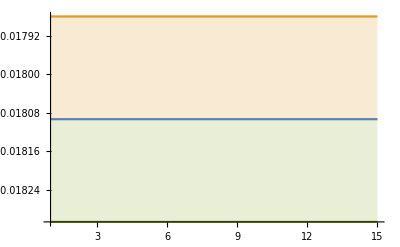

```mathematica
Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,15},Filling->{3->{1},2->{1}}]
```

```mathematica
SpoilHWFLOPlotN3=Show[Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,Length[meanErr2[[5]]]},Filling->{3->{1},2->{1}},PlotRange->{0,-.04}],ListPlot[{Table[{τSteps[[1,i]],meanErr2[[1,i]]},{i,1,Length[meanErr2[[1]]]}],Table[{τSteps[[2,i]],meanErr2[[2,i]]},{i,1,Length[meanErr2[[2]]]}],Table[{τSteps[[3,i]],meanErr2[[3,i]]},{i,1,Length[meanErr2[[3]]]}],Table[{τSteps[[4,i]],meanErr2[[4,i]]},{i,1,Length[meanErr2[[4]]]}],Table[{τSteps[[5,i]],meanErr2[[5,i]]},{i,1,Length[meanErr2[[5]]]}]},PlotRange->{-.03,-0.005},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]],markerlist[[4]],markerlist[[5]]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]},PlotStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau_{\\text{steps}}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3\\text{ (LO)}",Magnification->1.2]]
```

-Graphics-

#### QCD NLO - gauss

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={380,380,380,380,380};
NWalkers=200;
Nf4α1LoopBig={0.229421,0.229421,0.229421,0.229421,0.229421};
aList={1,2,3,4,5};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
csvData=Table[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"],{xx,1,Length[aList]}]
```

({mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.07085006415098133, -0.07145503636098419, -0.07006006615017292, -0.07021949687285582, -0.07293456893642192, -0.07302914057301924, -0.07324461595140708, -0.07326435205433199, -0.07086860913127396, -0.0715284317466564, -0.07097705705259234, -0.0714822014688735, -0.07227670487765557, -0.07255604194312643, -0.0729379857857849, -0.0724751860556593, -0.07214006996852562, -0.07472561819233237, -0.07624554246871018, -0.07456276531098548, -0.07670832217318149, -0.07747667348587754, -0.07409619286624768, -0.07591527953378571, -0.07537768817846159, -0.07747157893028818, -0.07740662985221619, -0.07764424747013816, -0.07574097067077237, -0.07523375856707085, -0.07829521011797556, -0.08076141811356774, -0.07698756041910072, -0.0747793245145047, -0.07558900091701637, -0.075648956711788, -0.07739411825679869, -0.08817087303118779, -0.08953111530632468, -0.07887154247239019, -0.07924289909392139, -0.07830407370195286, -0.07605118192779269, -0.0748335205437297, -0.07219149683392014, -0.07214913205841514, -0.07149412222941945, -0.07307211426133392, -0.07282146361830913, -0.07320147179275216, -0.07331008500395778, -0.07300021092793121, -0.0721460080453647, -0.07184170238531296, -0.07262070557264098, -0.07226836092313257, -0.07314411734389757, -0.07166871750969189, -0.07124169764833388, -0.07279408262010958, -0.0730525924001366, -0.07373341860335181, -0.07693901577969738, -0.07597116573780463, -0.07599994206674601, -0.07816124365260743, -0.0743894214376526, -0.0732886364402376, -0.07538833846282977, -0.07584130397889932, -0.07424139644231868, -0.07286968272186874, -0.07735914376456161, -0.07603145448997102, -0.07351016775971779, -0.07258579604268398, -0.07753971581334881, -0.07637636466907102, -0.07348729486262962, -0.07369133603207649, -0.07283356392371368, -0.07258329808104677, -0.07343226044465456, -0.07393999393311723, -0.0731613370510341, -0.07450772342887703, -0.0742218048835122, -0.07308119634206527, -0.07203031573080831, -0.07357348797473377, -0.07614966838218111, -0.07486680439222093, -0.07386545036070667, -0.07365914487493813, -0.07347283113193884, -0.07393989163922604, -0.07389123263170835, -0.07272953535991158, -0.07247911349259575, -0.0721259771406638, -0.0728974170591123, -0.07444593301421044, -0.07159759187912483, -0.07102349969273158, -0.07023368102626304, -0.06920498343407637, -0.0702599113634245, -0.06952889287032962, -0.0701226047343983, -0.07000962594673786, -0.070235445921468, -0.06947888706354191, -0.06939369554689669, -0.0679314012961561, -0.06777796008231597, -0.06780289815087773, -0.06710695138447295, -0.06751944985763053, -0.06792972428708136, -0.06688828764129846, -0.06638801834041576, -0.06627442037790711, -0.066790348477389, -0.06626467438040856, -0.06622783198156142, -0.0669352255031391, -0.0665190718971054, -0.06787878962824016, -0.06815746598791957, -0.06859974870073023, -0.06744569338891812, -0.06753245872390838, -0.06724351522476495, -0.0677907776860588, -0.06800622650332575, -0.06838085042995183, -0.06819724356414239, -0.06690140868483001, -0.06631179472807588, -0.06684420078426598, -0.06659860556882873, -0.06650587354954852, -0.0656108711828309, -0.06592399873596473, -0.06653574958817543, -0.06784964013699869, -0.06800409672250844, -0.07006493781050444, -0.06825295352986316, -0.06815660907270485, -0.06704588674358153, -0.0677058465517928, -0.06785950788629914, -0.06913519119137321, -0.06904881385269768, -0.06837777229503945, -0.06803496266532598, -0.06733199155442098, -0.06735366931371133, -0.06701724935076081, -0.06675786813270213, -0.06712463388916275, -0.06812198874653867, -0.06806414384869071, -0.06872881173129892, -0.06858883416756502, -0.06860564496913739, -0.0685634665087882, -0.06893098180488134, -0.07131594141767857, -0.07451988432888426, -0.0741612926528827, -0.07315075107362723, -0.0730564826232484, -0.07468613937074102, -0.0731276126906054, -0.07353420838161426, -0.07249451574158318, -0.07212589195140542, -0.07146783926436164, -0.07724985361148753, -0.0728358425958702, -0.07327644578901685, -0.0729704029731949, -0.07577405288548324, -0.07558337379977716, -0.07443247301930304, -0.07257040336089587, -0.07208773906292261, -0.07210098005119724, -0.0741621721908112, -0.07160011901459741, -0.07057265866960247, -0.07231238092645412, -0.07169638067983855, -0.07202729527436585, -0.0724481850394217, -0.07211648141050447, -0.07282377319459964, -0.07129344348003172, -0.07098182285991216, -0.07010497971732581, -0.07061867544450406, -0.06959704925248357, -0.06892075460150131, -0.06864210394973258, -0.0680712640042627, -0.06804346724736188, -0.06889814202466389, -0.06971824676380041, -0.07046541318515127, -0.07002495517801002, -0.0707566386407062, -0.07039055603641817, -0.07029563547661148, -0.0697600121305017, -0.07018613219099697, -0.0694949259528537, -0.06954786175557322, -0.0697784324677018, -0.06924991894386355, -0.06945685462866029, -0.06932665073985093, -0.06943644230875733, -0.07059633155096456, -0.07080676006583737, -0.0722526588760509, -0.07321391232153118, -0.07342803684264661, -0.075751174379324, -0.07555429409468141, -0.0780156676468893, -0.07608203367691281, -0.0736580958999896, -0.07168455806078614, -0.07201124359616812, -0.07378318015559904, -0.07349544333496857, -0.0733184492956741, -0.07263871417278925, -0.07163526199562038, -0.0720315018268786, -0.07154984239489323, -0.07141763154143958, -0.07090963420685562, -0.07238023235310084, -0.07133765662718704, -0.07163967579521496, -0.07237376481027763, -0.07245655256438768, -0.07256892630959318, -0.07370113214587339, -0.07346588602352792, -0.07282894142046929, -0.07257511391484886, -0.0714929244358686, -0.07113174565113127, -0.07077634781976608, -0.0716982648839647, -0.0716469449124981, -0.07195781866097357, -0.0727052561077625, -0.07235702316332956, -0.0733634655634266, -0.07362941198105037, -0.07332734244611369, -0.07246800297046238, -0.0734697966569345, -0.07352127506533263, -0.0768509107755556, -0.07712124471105491, -0.07731295621285836, -0.07720162922352439, -0.08022997191781286, -0.07769627403288384, -0.07558597682480485, -0.07391783911756956, -0.07393555110444898, -0.0768185436567748, -0.08497367635092881, -0.08041596467203928, -0.0796211282320295, -0.08118944210899882, -0.08000113057911905, -0.07777161009790065, -0.07757957597839112, -0.07791315728071524, -0.07859511584471728, -0.07833884721449902, -0.07837275494016697, -0.07709947820157555, -0.07634849101090348, -0.07537378912481374, -0.07660535809869606, -0.0763347438896354, -0.07517287340027853, -0.07426923034331183, -0.07496378236484498, -0.07458450451895499, -0.07433619232743409, -0.07468612525228857, -0.07451556156970934, -0.07278967924949152, -0.0733434845010487, -0.07544207964141401, -0.07801296080599326, -0.07780129065034584, -0.07976918351675134, -0.07810470851415181, -0.07532745606578145, -0.07564715841223654, -0.07760073690278299, -0.07715151720402959, -0.07459247329247623, -0.07488204266867114, -0.07360307583771848, -0.07294065182751697, -0.07386327891089646, -0.07267706938639418, -0.07366546969239987, -0.07271816022887766, -0.07167659714627306, -0.07061010273915913, -0.07141444418101356, -0.07070887859982164, -0.07134408331844327, -0.07129532164729936, -0.07145212886801587, -0.07070335261501498, -0.07084101125734436, -0.07058335643625951, -0.07018107261964304, -0.07068769504614425, -0.07302335816864093, -0.07262844501129459, -0.07187761741170934, -0.07066059266519188, -0.07071120304627321, -0.0714708031803571, -0.07194316452935448, -0.07270160507697046, -0.07355071279296374],[0.0028093730143950346, 0.0031340685557609974, 0.0024428060507602897, 0.002675990788606096, 0.0035310916110163067, 0.0035455414194317312, 0.004115265193659863, 0.004270152351891434, 0.003098184109530155, 0.003398369266865106, 0.0031181996929732477, 0.00330137385138466, 0.003418800084435505, 0.0039217207731995565, 0.003881016331026856, 0.00390037410559201, 0.0035637795993122045, 0.004980235555190182, 0.005653643610117388, 0.004562675221271215, 0.006132923290863124, 0.005992011166091205, 0.004110924591583325, 0.004993144736531991, 0.005141957694759715, 0.0055860907163838, 0.004851524397230612, 0.0055636293851990095, 0.004809850830774655, 0.004435657427159924, 0.005704852072991653, 0.008042381681957875, 0.006089740097036258, 0.004530048617479821, 0.004757059026935016, 0.004798366727256551, 0.0054256516940648794, 0.014092168967726786, 0.014655681729813536, 0.006130405553278149, 0.006203170708947937, 0.005755527877205726, 0.0046674213502061685, 0.0041548315746282715, 0.0030041087632521287, 0.0029813429574567438, 0.002632427006900628, 0.0031385387504790454, 0.002941054978842086, 0.003204930559157837, 0.0031947211143113236, 0.003050373079062811, 0.0027091336072158365, 0.002606126371799766, 0.0026364599255941684, 0.0024166556162665944, 0.002854470446147839, 0.0023890348117395366, 0.0021479459312823005, 0.002489362296681998, 0.0025181800999938553, 0.003245432940479952, 0.005050876373371216, 0.003793256334510939, 0.003806440107641877, 0.004838717356614361, 0.0033560577359877616, 0.0029441316955796074, 0.0040671982994556575, 0.004796873921117934, 0.0036795953155076464, 0.0032766160823616075, 0.0065529396901441465, 0.004418063927440491, 0.002887604476764531, 0.003310881629221698, 0.005746819167969176, 0.004086158317257029, 0.0035769923064920637, 0.003438293991822333, 0.003049203044561269, 0.002749902801972803, 0.002809652692230392, 0.0028691905110658626, 0.0027261932194361815, 0.0032172858798036256, 0.00288785362499501, 0.0022296344438656073, 0.0021079798988566634, 0.0021914895336197933, 0.0032363428001146353, 0.0026326878796397815, 0.0023459363234716746, 0.002360401292111256, 0.0026418395469702356, 0.002868652154807058, 0.002948706330472843, 0.002576605286419194, 0.002443190251030788, 0.0027066925878200154, 0.0026991101171614145, 0.003762329626712914, 0.002531344718976716, 0.0024925606508961052, 0.0023563059112948997, 0.002140189334849344, 0.0023508127237691122, 0.002054530509513305, 0.002234960478369875, 0.0023005656898688904, 0.0023439325631602424, 0.0022005594864053777, 0.001965809816810705, 0.0018085401724306424, 0.0017851967730310038, 0.0018452591754941747, 0.0018561927040934491, 0.0018201255601756486, 0.0019349280038767776, 0.0015862983105686427, 0.0016521009021465715, 0.0016100922030451664, 0.0018119691800400873, 0.0015562273473153862, 0.0015177536131344477, 0.001949958401175632, 0.001766312064113565, 0.0025294614754942444, 0.0021080702624531994, 0.0022070085100278467, 0.001973716093828972, 0.0018906322038608904, 0.001762794914017398, 0.001877064548043882, 0.0020165296651853556, 0.0021145634442865744, 0.0018430457740519625, 0.0016589251145910412, 0.0015821123937528848, 0.0015370531825311003, 0.0014983826822822968, 0.0016095748647061742, 0.0015347183898757417, 0.0017633107804002049, 0.0017956454709376559, 0.0019535759990080303, 0.0018391774384679631, 0.002906258872110052, 0.0017430984315566927, 0.001964059959477322, 0.0014515896703520088, 0.0014556698927577299, 0.0015002660806478143, 0.0017267861379088394, 0.0017483856788275659, 0.0016238982301682123, 0.001521792290215921, 0.0014509895358934437, 0.0014212854548641552, 0.0016576126390469182, 0.0015574470151004565, 0.0015819621752090679, 0.002004491750638409, 0.0018506843514203063, 0.002009842616426377, 0.00201214025224078, 0.002265846175901993, 0.0024939800644895728, 0.0024389227037480833, 0.003067902394744302, 0.004260896683188321, 0.004101697110398047, 0.003543252599717566, 0.0033575652089087716, 0.004299529437937927, 0.004247497343249964, 0.004121567029436838, 0.0036905978489360563, 0.003524287678117489, 0.003255623831215956, 0.006287493953152462, 0.00399566765436099, 0.004206961685473173, 0.004166638400036308, 0.005219336437418444, 0.004928512035944548, 0.004497294315367423, 0.0033391956406021595, 0.0029283950262606754, 0.0030655271468709236, 0.004800166635805038, 0.0029673068782575585, 0.0024559830632335006, 0.00269142821922563, 0.002679517239543422, 0.002782728631778961, 0.0033935238850216964, 0.0031295728369242232, 0.003292964954918988, 0.0025435245168001245, 0.002514085639412144, 0.002227999482072133, 0.0023216947266668886, 0.002080817299433705, 0.0021337835522238216, 0.0016839448735192733, 0.0017068285724469215, 0.0017012306733697944, 0.002263977682273756, 0.0022795215682732883, 0.00263934664702817, 0.002329257588273852, 0.002493170368559426, 0.0023141028619835173, 0.0021939432296240883, 0.0022213803223207736, 0.0020954704185426457, 0.0019790466031993715, 0.002037420122079286, 0.002151264961727082, 0.0022055265000463925, 0.0022247685816281925, 0.002238338047166664, 0.0023688254424783233, 0.0025847034830064675, 0.002539253927034735, 0.0029341609500240376, 0.0030666973243094154, 0.003105973210023676, 0.00420079317458281, 0.004017702745554994, 0.005868987945474691, 0.0043930329097061965, 0.0034254061725645098, 0.002602237923947415, 0.0026069175225014035, 0.003138023662097038, 0.0028516721895507123, 0.002696224541671151, 0.002801905305671798, 0.002076804206576502, 0.0020547390458006643, 0.0020944782046780764, 0.0020186302158439542, 0.0020507414763403344, 0.002294475781686558, 0.0021359435542896185, 0.0021717264579361544, 0.002289565811606719, 0.002528947722399795, 0.0025604119921395292, 0.003467145614575516, 0.0030006734237287514, 0.002647026872178127, 0.0022251461018415186, 0.002373839361836911, 0.0022323377001492195, 0.0022436418210174543, 0.0024332444148690373, 0.0021219271091799585, 0.002294333890060069, 0.0025351721187748476, 0.0025243392017689653, 0.00267704522371592, 0.0027281803400109874, 0.002862285909400942, 0.0026939168833872203, 0.0028830702856095856, 0.0029393190376152296, 0.0046013013089638115, 0.004170114407341288, 0.0037081757446595174, 0.003701626095050141, 0.004335027407339472, 0.003558592288227881, 0.0032143375478169353, 0.002826093776665676, 0.0030876852425805864, 0.004270023220895186, 0.010586947986472245, 0.005528506973444244, 0.004420106438587315, 0.0050457155762496445, 0.004229974944239533, 0.0036620810573265356, 0.003449186870495807, 0.0040016844701944885, 0.004231831034301356, 0.004641378314433796, 0.004967930497326409, 0.0038430747162873182, 0.003688098434873981, 0.003231076770870595, 0.0033813207495490957, 0.0030777401444562298, 0.0026615606930855524, 0.0024883437065343554, 0.002614368278866447, 0.002595073726541127, 0.0027285870851159783, 0.0030576638107925225, 0.00300137464721754, 0.002744082099685492, 0.003257834845685298, 0.004005444740152016, 0.004744961583503114, 0.005080991165641533, 0.00518665371644961, 0.005192639991740145, 0.004122945244366035, 0.0038388958477924796, 0.004401186451031579, 0.003944911076248995, 0.0033113025417153183, 0.003148428282148696, 0.00289822179682213, 0.002567862845665757, 0.0030023177017638077, 0.002614530248101321, 0.002837096997032923, 0.0029070916304939575, 0.0028260106462219626, 0.002613945493778877, 0.002945792469621465, 0.002866280862912374, 0.0029958056092664236, 0.002990730637276221, 0.0034214718968590247, 0.0033952436929533133, 0.0037136998310631003, 0.003566015877283832, 0.0028608321224945945, 0.003037705386005028, 0.003680009755725528, 0.0033637080485791324, 0.003077432451405124, 0.002755718139478518, 0.0026116258472427163, 0.002725730779479827, 0.0029965550427124466, 0.0034229615913789653, 0.0034721037065924614],-0.0662094,0.00042585,0.59041}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.04628658273194879, -0.04659161502873505, -0.046961314623115244, -0.04670061810874436, -0.046724153417188635, -0.046719462361940314, -0.04643709767346699, -0.04666993593691184, -0.046660108787339644, -0.046654692684222517, -0.04658151783617961, -0.04669809500739859, -0.046904011284079776, -0.04682832861969816, -0.04667125183574615, -0.046744760592407716, -0.046684348276851736, -0.04746154107726318, -0.0468773758798583, -0.046869070595852526, -0.046997712204632225, -0.046979186888315434, -0.04694499949241759, -0.047019704240248025, -0.04718203325305918, -0.04745951554233787, -0.04740841119218764, -0.047356913519479696, -0.04725990710883205, -0.047172044593734364, -0.047340657731390956, -0.04702947108565404, -0.046618235382093115, -0.046632109055916304, -0.04658035173851737, -0.046901328228649314, -0.04730010275844466, -0.04760466401453789, -0.04728053378100949, -0.047354301006337696, -0.04752417031220819, -0.04728612040535701, -0.04715505656300789, -0.04736581939110327, -0.047145618309666, -0.04713720452283341, -0.04711457363701416, -0.04706172338859709, -0.047303574762867166, -0.04749315579273385, -0.047243997199424875, -0.0468924141082507, -0.04694183324770506, -0.04704320436525691, -0.047245567960593524, -0.04756437952166806, -0.047494156984903294, -0.047474546796044494, -0.04756074448004819, -0.047371418003909364, -0.04783351386628663, -0.04755237811959736, -0.04768117113148616, -0.047620761561896714, -0.04772782433017122, -0.04749364978850324, -0.04750406747148574, -0.047738821127484996, -0.04760436663191025, -0.047739566282116605, -0.04807958909680743, -0.04788610877378882, -0.04758325887540932, -0.04758546624149454, -0.047705856934934246, -0.04775535983693087, -0.04775897812253735, -0.04792625010718333, -0.0478352264420352, -0.04797244026957871, -0.04814913117698738, -0.048419263214753594, -0.04830791575098987, -0.04831002444744752, -0.04869357104470956, -0.04846086979708156, -0.0479957419232293, -0.04832874816649294, -0.048281911931885135, -0.048027903416083116, -0.04794760529294522, -0.04775706592445725, -0.04813608639874302, -0.04843105296984002, -0.04883049791453891, -0.04899712884340506, -0.04891560585674229, -0.049141803451773304, -0.04952960710654696, -0.04986731693489434, -0.04991053011415688, -0.049788687787269845, -0.049948129703460346, -0.0499484207771565, -0.049825026356869834, -0.049371139944459574, -0.04925269932020444, -0.049390789237284294, -0.04938810820719682, -0.049435405231760446, -0.049480911353353654, -0.049046582682514606, -0.04879453806136893, -0.04877525432735934, -0.048967345794538986, -0.04885675861224831, -0.04881849290133802, -0.04829984197971138, -0.04842949823127285, -0.048524130990559355, -0.04855763610676436, -0.04844138124828371, -0.04832256793338905, -0.048503603757104254, -0.048242597329562015, -0.04825378096472853, -0.048187524346878, -0.048714003889232846, -0.05004148976942388, -0.05396370480965964, -0.05160261024397277, -0.04961096821250886, -0.049781391681971855, -0.04917405786137631, -0.04914778581826246, -0.04882075204868958, -0.049081647243875814, -0.049087697952487006, -0.049150825236995765, -0.04945748179714485, -0.04970662706493695, -0.04975954372624099, -0.04965876956910445, -0.04966751983892147, -0.04985644538957722, -0.049904249704299866, -0.04981152654388798, -0.049843384334509626, -0.049882313094632355, -0.0499661263620279, -0.04978563861000036, -0.04999200066625428, -0.04971286049840587, -0.04992997494712537, -0.05010000183826676, -0.0497058630564572, -0.049805756075212364, -0.04993205564833946, -0.04993597400931211, -0.04963341117729098, -0.04961334785766017, -0.049730947387616145, -0.0496454753814356, -0.049847445793390045, -0.05027331048240055, -0.05078264351007576, -0.05120549067160053, -0.05083306301152572, -0.05056095708700268, -0.051148118407770025, -0.05164254611803362, -0.05232093855707835, -0.052277951561414404, -0.05193013755477738, -0.05261331994061891, -0.051988547843687935, -0.05191045530194334, -0.051848073378204663, -0.051912533854367914, -0.053952171015874635, -0.05400281537739278, -0.05395595304734575, -0.053261839828121965, -0.05273377383894938, -0.052921693483575116, -0.05263590572620619, -0.05251341402983344, -0.05247423682726059, -0.05227137916838082, -0.05208465512045883, -0.052340498964181956, -0.051630934639872346, -0.05208779726069795, -0.05165414481483006, -0.051794736775756245, -0.0516633794777173, -0.05151771396666677, -0.05172490412046452, -0.0510911630834023, -0.051931730733294046, -0.051731955783460536, -0.052216341088926504, -0.052598666705890036, -0.05195590723957418, -0.0514255561340612, -0.051139928002171695, -0.05142548142471039, -0.05080701785039249, -0.05097979927907833, -0.05092246903056528, -0.05163606818516555, -0.05278353685048245, -0.05280314354808534, -0.05283771416047169, -0.05323062528307295, -0.05269168090502893, -0.053519750805168055, -0.05310444825881844, -0.054358039485625, -0.05393703014903153, -0.05343919288466669, -0.05380297654698642, -0.053018172907800566, -0.0536339259936793, -0.05305497851210521, -0.05295765617109105, -0.055015625007980434, -0.05443754812244736, -0.053891783091514, -0.05430692848848411, -0.05319137826101686, -0.05453988372001593, -0.054578742264001424, -0.054643027830985985, -0.054782759658949194, -0.054010604592238144, -0.055417701277671996, -0.05740183130520622, -0.059492453212110996, -0.05650849114780158, -0.05629281706616047, -0.05547461142793883, -0.05503762709474688, -0.05458874068621923, -0.05403540919655472, -0.05373792607488467, -0.054388490214287585, -0.05420507021941836, -0.055399186484343124, -0.05627219829666458, -0.05533140074218631, -0.056368862972910216, -0.05516129822831311, -0.05642739737869, -0.05632370212106661, -0.05641226636831801, -0.05575834282215552, -0.05583818938108425, -0.05496666785430915, -0.05539974018822432, -0.055165591004060446, -0.05425486309295177, -0.05480724173195661, -0.056171667558843744, -0.05610501417170031, -0.05555047221611358, -0.05502816444567398, -0.056110324045022704, -0.055622674898620744, -0.05645903351901776, -0.057620516568319805, -0.0574926665271181, -0.05793468395369549, -0.058435110557721236, -0.05878655154917893, -0.058070854403449675, -0.0584742957253987, -0.05904648519461848, -0.05881447255473548, -0.05857862178533391, -0.05757490121025323, -0.058105725136388064, -0.05787040200102381, -0.058670573712431326, -0.05672000412764189, -0.05828041556431316, -0.056945074714476664, -0.05882379848316191, -0.05971256838849622, -0.057995618600674814, -0.058635690159896864, -0.05835072201265101, -0.05786337821075071, -0.057938079566999555, -0.05907947789806053, -0.05842304276859138, -0.0575941525318163, -0.058018727296840926, -0.058658360389931524, -0.05870335541945864, -0.05864609619592144, -0.059351070637263595, -0.05965752415762254, -0.060015780149595896, -0.059743610282752546, -0.06060430391064589, -0.059752850145853034, -0.058174013027351854, -0.058184163895908185, -0.05823237028386361, -0.05900702731655412, -0.058953853267494895, -0.05816403019079094, -0.05695583720347383, -0.05705634616315006, -0.05810998897967156, -0.05847282495392151, -0.058655500512946344, -0.05866019686866444, -0.0609533951553161, -0.06142444221209781, -0.05957955142088101, -0.05903906444879584, -0.058720325339329624, -0.05855858621797212, -0.05885385773498395, -0.05835409950154518, -0.05845454794414547, -0.0591180680244682, -0.05943851114465423, -0.05967892580422692, -0.06019053429032974, -0.06068870204471836, -0.06098056721745732, -0.06059568493719005, -0.06214244443416192, -0.06129174960236556, -0.060015170236853065, -0.06145790275521418, -0.06237801472565777, -0.06327309653519006, -0.062202325550440835],[0.0011835972705063118, 0.001254011200318403, 0.0013868019630262271, 0.0012759339246331573, 0.0012777367849045194, 0.001282579098671536, 0.0011894666124355436, 0.0012497288657806944, 0.0012375337976062541, 0.0012323004691819014, 0.0012096846574244885, 0.001217766758673371, 0.0013081579714322889, 0.0012909473638719792, 0.0012731632359221003, 0.0013636408524424274, 0.0013782420952927167, 0.001781241428825897, 0.0014475503394404381, 0.0014897036150955823, 0.0015161943139939415, 0.0015278032135558205, 0.0015572839186501735, 0.0014920331179010095, 0.0015773371581156454, 0.0017102453684419826, 0.0016310812220706613, 0.001564054685178607, 0.0015348517055422516, 0.0015236256637879235, 0.0015898942427480165, 0.0014833692050149436, 0.0013913337936199129, 0.0014396961983252064, 0.0013648222726641694, 0.001469515966973304, 0.0015860821596318257, 0.0016391071716816807, 0.001464231344152902, 0.0014798282483157203, 0.0014735935269993572, 0.0014239217420623535, 0.0013988030767408143, 0.0014523071732523193, 0.0014507487641672327, 0.0014336581354359355, 0.0015232202477254643, 0.0014778296904210241, 0.0015345427826459637, 0.0015709257085189362, 0.0014091757688142526, 0.00132085397896912, 0.0013516125579347144, 0.001364953609360199, 0.0013918034084315965, 0.001458025661771995, 0.0013973134555500092, 0.00142574267869017, 0.0014001626771265273, 0.0013552153748409418, 0.001462708815647425, 0.0014078698802936509, 0.0014118011622623512, 0.0014537179185809194, 0.001423518490160096, 0.0013486846974850057, 0.0013615171526426904, 0.0014486632674269638, 0.0015080591072114344, 0.0015138792466198902, 0.0015391485670744373, 0.001499598029063582, 0.0013951084574320366, 0.001429136345265727, 0.0014795256192493844, 0.001522060846129865, 0.0015190695061803334, 0.0015659182049951414, 0.0015047968391235526, 0.001485907047627473, 0.0014774048494389795, 0.0015791060581686362, 0.0015750374005451097, 0.0015031895325438977, 0.0016611528604390299, 0.001592991985431782, 0.0014238290373637615, 0.0015565677664500246, 0.0015122803213747083, 0.0013977663070195046, 0.001350753437423321, 0.0013429658499624563, 0.001390268523726922, 0.0014547302795766017, 0.0014907229877550551, 0.0014827189590216814, 0.0014196245837066648, 0.0015140412854209883, 0.0015990888917280853, 0.0016573290361035925, 0.0017429831498960752, 0.001735256043212108, 0.0018284149260165256, 0.0017771051033369603, 0.0017626359074746935, 0.0017184760133453565, 0.0016626334094348378, 0.001708840445201379, 0.0017413562070900744, 0.001818460066736626, 0.0018426507949335048, 0.0016989996724370614, 0.0015762613742951001, 0.0015350966415065284, 0.0016129549484929964, 0.0015865382834577282, 0.0015355941519784534, 0.001404883572762026, 0.0014591247676311952, 0.001528946321381311, 0.0015238448114135647, 0.001454536788211465, 0.001398350343835174, 0.0014747316069357152, 0.0013578966903465444, 0.0013841958988458501, 0.0013351532347911793, 0.0015329432544827577, 0.0024794794142866707, 0.005963329122090325, 0.0034390923261479072, 0.0017692814423388695, 0.0018031407851639646, 0.0014528468815735117, 0.001368735925985484, 0.0012864336514250272, 0.0013360531509747546, 0.001339022801315556, 0.001345943901401464, 0.0013656081444234213, 0.0013894836024214686, 0.0014476218761828633, 0.0014676600041540924, 0.0014701672985479705, 0.0014619685662985264, 0.001400045349891713, 0.0013431411839075198, 0.001350182309291975, 0.0013814355242166446, 0.0013677282706285184, 0.0014032375587605583, 0.0014053418148004112, 0.0013734705893743372, 0.0014123607111710523, 0.001435306375366895, 0.0013685470727389263, 0.0014005689369632301, 0.0014822866021457163, 0.001477518884007464, 0.0013920616764001381, 0.0014081708376243495, 0.0014314388869683125, 0.0014427091567338973, 0.0015155891350783631, 0.0014695999653599877, 0.0016030905739168857, 0.0018240773616164784, 0.001679532617966279, 0.0015800684423699983, 0.0017642883214372676, 0.0019072659668171925, 0.002177138056526957, 0.002261760883044259, 0.0021270073946979815, 0.002365549273377781, 0.0019992437300177936, 0.0019067090664867399, 0.0019214426379209558, 0.0019696927999217394, 0.002997795469440104, 0.002758468549380725, 0.0026525305290034658, 0.0024566115192666657, 0.002271705399133626, 0.0024592892004901908, 0.002146119990800784, 0.0022030854431947834, 0.0020981042974705555, 0.002055931054574174, 0.0019441713124802036, 0.002123431677190713, 0.0018678016442428991, 0.002038338696285143, 0.0018953625380948341, 0.001970266458676147, 0.0018679198450334725, 0.001787206421711802, 0.0018667855775358632, 0.0017708779812717996, 0.002097253024091209, 0.0020120214291255304, 0.0021140965531977877, 0.0023687342540404453, 0.0022882102078785986, 0.0019994968510302336, 0.0019597551970288994, 0.0020522944996889075, 0.0019554807915101316, 0.0019485563036032078, 0.001932890834585749, 0.002247139708337523, 0.002901833909306234, 0.0027696917981964585, 0.002570709844123091, 0.002561418699594155, 0.0024024813012331592, 0.0027032291864015168, 0.002431089505444725, 0.002784041321865823, 0.0026084840326423167, 0.002444470034025297, 0.0026009405445104683, 0.002312977412344951, 0.0024886778634120935, 0.0022088091037459484, 0.002171728221394026, 0.003475409451023521, 0.0030077099985031486, 0.002780565883020447, 0.003021686006978403, 0.002503644692645849, 0.0029651921772640664, 0.0028642672344514723, 0.0029027778601296832, 0.002980250822064115, 0.0029927177408729665, 0.0038302729498442354, 0.005041852529992703, 0.006547558336396498, 0.0041153319226521195, 0.003777435417503446, 0.0032768918225909967, 0.0031617074180541153, 0.003032744849657402, 0.002703599927889663, 0.002491754570697651, 0.0028437673155080633, 0.002879884361551355, 0.0034915187252611748, 0.0036897147405060013, 0.0030836376233959618, 0.0035622356687633142, 0.003232006276537916, 0.0038566050933640256, 0.003819930096871487, 0.004062402805838807, 0.003663550810562373, 0.003232962812265085, 0.002878621698683886, 0.0031102317620054117, 0.0028309026192882497, 0.0023614670000971206, 0.0024713149205008132, 0.0029139235488027312, 0.0026616527692221057, 0.0024936152768712696, 0.0023936118311133985, 0.002688746122054572, 0.0025082834338653504, 0.0031537610444124834, 0.003302049569255257, 0.0033419348537451275, 0.0037459411724703705, 0.0034854172237270098, 0.0032521651750539123, 0.002966069528203226, 0.003028391503303633, 0.0033306974505684884, 0.0032754087276348964, 0.0033038922227849555, 0.0027931198029748213, 0.002908148103220795, 0.003005240517897274, 0.003320493006120538, 0.0027013778875455844, 0.0031982655084108803, 0.002839436892595022, 0.0033855781325297023, 0.0036487870517302443, 0.003136656339382551, 0.003247790833706264, 0.0031352202928557407, 0.003135961950233861, 0.003107874752907471, 0.003936737273776242, 0.003742902420089831, 0.003430900603729798, 0.0034661659259538203, 0.0037610587882654415, 0.0037343393285711435, 0.0037015427461195988, 0.003940761278672933, 0.0039971242715588495, 0.003906559489482072, 0.0037667869172254976, 0.0041466885645116735, 0.004334691993149868, 0.003449255453663708, 0.0033892131129026875, 0.00318075857953501, 0.0033416011804063483, 0.003333945738927714, 0.0027330766905385865, 0.0024632150703959082, 0.0024525881152829446, 0.002767017515672289, 0.0031282378427878697, 0.0032978083405311893, 0.0033922310482891165, 0.005167970914044466, 0.005108986469117477, 0.003806244632112009, 0.003177387660970273, 0.002940162000100507, 0.00272680104364135, 0.0027421936463813534, 0.002733852562034548, 0.0027763377937681973, 0.0030646704043205994, 0.0030395228226048026, 0.0031721502351631983, 0.0033771822400669223, 0.003600530928429706, 0.004028546248598317, 0.003821984714120423, 0.004261092660500846, 0.004132064339798906, 0.0035277775286855916, 0.003811736674352017, 0.00482830398478078, 0.005137846520987615, 0.004385114064051449],-0.0450731,0.000657896,0.311533}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.036559365607199315, -0.036664647617676245, -0.036613460380698265, -0.03630285472364334, -0.03629921396831698, -0.03646290688409406, -0.03658243080854997, -0.036516937468190104, -0.03647111750666534, -0.0365002865214385, -0.03672599971533545, -0.03673425743180457, -0.036625028712896614, -0.03641054507665286, -0.03646914604171674, -0.03669264002149807, -0.036859765553416975, -0.03687280043072691, -0.036851790920345295, -0.036572114315750574, -0.03751238873385374, -0.03751613934442014, -0.03799596808185098, -0.03755306882471961, -0.03788688047815561, -0.03756052726321952, -0.03784035772259854, -0.03781024408427397, -0.03762519052796918, -0.037284095973436425, -0.03724050993349069, -0.03746914850951561, -0.03761966377773828, -0.037525066224342145, -0.0380755478438723, -0.03810767207511097, -0.04016143593460095, -0.03924714236885408, -0.039993748314601986, -0.038564358463019886, -0.038833114196079245, -0.03871884013052623, -0.03847882525128307, -0.03863209552802184, -0.03913012565478217, -0.038390631184323495, -0.03872046393523462, -0.03864660670963058, -0.03867458793515855, -0.039233183528724624, -0.03870451266255699, -0.038488266678341654, -0.03872881677029368, -0.03876553348885048, -0.03855374201167745, -0.038435552398601976, -0.038274939635317994, -0.0382977216148475, -0.038569723690448844, -0.03883147990818312, -0.03918334340421493, -0.03917974821878762, -0.03888560499649646, -0.039124242300264366, -0.0390993202147139, -0.03912494326060505, -0.038871193235238244, -0.03863722179789531, -0.03844906334371673, -0.038918132315906136, -0.03907909053511559, -0.03902638183099077, -0.03927044366100231, -0.03960676232713307, -0.04050202249776645, -0.04092186438502698, -0.040456688679168566, -0.04029838919030893, -0.03998452399753977, -0.039783928966188355, -0.03966175481970153, -0.04001010518951729, -0.03962468615281772, -0.03972510890672781, -0.03954684742407009, -0.039403238695118824, -0.03923255469829956, -0.03933027382655882, -0.03914425153469687, -0.03916109462307455, -0.03891472319661675, -0.03910220130293562, -0.03931745489104451, -0.03960482424268055, -0.03950992049039493, -0.03941635524775231, -0.03967577112372715, -0.03995582406832444, -0.040151974761170973, -0.040524974919457286, -0.0405023017654271, -0.04032025111505006, -0.04008089044145206, -0.040208873111739145, -0.040389604352138425, -0.03949230111564371, -0.03987223330606733, -0.040193651111700236, -0.04073418665877986, -0.04260325825474807, -0.04460324294857606, -0.04569215348082959, -0.041187490406943444, -0.04043130916236832, -0.03992553440506714, -0.039589310429611384, -0.03980933806140591, -0.03934140712219737, -0.03928719279455687, -0.039115039305776665, -0.03896750438548507, -0.03892188451701852, -0.03890431801477105, -0.0390389776601582, -0.03894001007667649, -0.038875990357921705, -0.03886331895246193, -0.039062537958602324, -0.039251870825236304, -0.03945180426533428, -0.04218644591537122, -0.04060228711114802, -0.039667979982203644, -0.04119927596439459, -0.04278637615190481, -0.04026758989595008, -0.03999819088106505, -0.039454962291515565, -0.03916973264069267, -0.039327352446857824, -0.03974211185105454, -0.04007879621035423, -0.04007058541750622, -0.040021253392233176, -0.040401860093888346, -0.040491339503156316, -0.04083301125888095, -0.04083316186711616, -0.04105974297288548, -0.04129341187373611, -0.04173405895057771, -0.04147607248907584, -0.04165635807605247, -0.041089764967101844, -0.04128670842034716, -0.041293484977747166, -0.041446501211006945, -0.04109149797228173, -0.04069164678855863, -0.04037922191478907, -0.04065623852765925, -0.04074988505102518, -0.040845505437153214, -0.0406199781349659, -0.040911341939988854, -0.041229499729600785, -0.04140465348550226, -0.04110937733553608, -0.041064472145875504, -0.040921200862271724, -0.04084870963652727, -0.040785405094640764, -0.040659502752944214, -0.04083394863813659, -0.04084168238960306, -0.04091825812708569, -0.04096811536829364, -0.040786073587118304, -0.0407224938565834, -0.041078448578724655, -0.04149510488708252, -0.04152246656978222, -0.0412641067021377, -0.041217709715471576, -0.04154740820286576, -0.04151240437852393, -0.04220746897507103, -0.04206732849723094, -0.041902260613526615, -0.041559192853301806, -0.041190998683356544, -0.04124575776975587, -0.04114192066550372, -0.04131857014443521, -0.04162357821081512, -0.041289247825554626, -0.04132965670051501, -0.04148465458450333, -0.041366776255689616, -0.040905415803584255, -0.04080626050611578, -0.040765650300711956, -0.04095595917467386, -0.04087144092458818, -0.040973246437000635, -0.04079604637289115, -0.041075481612372525, -0.041210032521602054, -0.041149375273867646, -0.041115286153476226, -0.040861414055252405, -0.040914864834261454, -0.041243208033159694, -0.041603048911416245, -0.0416171902265329, -0.04126850643661882, -0.04172375477194375, -0.04153170337817881, -0.04151465067635839, -0.041283145373157304, -0.04146798171644895, -0.041288673507746024, -0.04135746844219604, -0.041555515564857565, -0.04167044886621733, -0.04189527664708975, -0.04186033460935053, -0.04219119993359436, -0.04205940538007439, -0.04198817323251248, -0.04206930059528708, -0.04218274193891042, -0.04184467788244254, -0.04201607628996954, -0.0421646776373054, -0.04205231442037511, -0.041879889219428056, -0.041733876523164, -0.041796764868060034, -0.04195913143420851, -0.042069372446583965, -0.041843245078590476, -0.04188402781549539, -0.04206355556511396, -0.04202996373309902, -0.041874604880082475, -0.041944731911745255, -0.04201358475129977, -0.042198860810002695, -0.042481738826994735, -0.04233091536944081, -0.04212599133236936, -0.04226776762202283, -0.042302451262556544, -0.04183856499621883, -0.04179933962271657, -0.041588444036893726, -0.04202546313936816, -0.04173861095589542, -0.041867752958894305, -0.042207071080620155, -0.04186086810806806, -0.04196736576000672, -0.042195421199222406, -0.042522535043155514, -0.04234523188937519, -0.04255654419092169, -0.04258525564074641, -0.04293553004844249, -0.04280314148828993, -0.04325876111356315, -0.043469772192224025, -0.04321392915740975, -0.04346432032451846, -0.043813583559331994, -0.04381751850288343, -0.043852351245314954, -0.04371208800736007, -0.04359634275013837, -0.04416317357809619, -0.04416345715231883, -0.04377561513610928, -0.04347444181865226, -0.043458807925870716, -0.04309018260681269, -0.04333371197042866, -0.043360015069286634, -0.04404176441709871, -0.04386140081144462, -0.04364013164711783, -0.04394471761730197, -0.04421660810568211, -0.044091935684181766, -0.04388807961405672, -0.04387959701655897, -0.04380970120180411, -0.04407039452898176, -0.04395984161201213, -0.04395527723028896, -0.04416194636184498, -0.043927650291882114, -0.04400000576225828, -0.04392211061623369, -0.04423389164470274, -0.04374965620952616, -0.04379729697349838, -0.04379676254790461, -0.04367438957910026, -0.0438929216724865, -0.04445090639829035, -0.044628255345712145, -0.04444999544618463, -0.044793205040179244, -0.04439477507926277, -0.04426916859021746, -0.04449415094889182, -0.04444583996907923, -0.044626676224730155, -0.04495723366714475, -0.04482210005426186, -0.04479098498523834, -0.044509419993644106, -0.04457479565922222, -0.04508491335415393, -0.0452307957328034, -0.04572643855943545, -0.04571758771474929, -0.046126016476648095, -0.04624524710844017, -0.046185330866333106, -0.0463023198390787, -0.04617394362081102, -0.04632647309722417, -0.046367620223934494, -0.0462041742298463, -0.04644357688496368, -0.046198307577202356, -0.046068860032505723, -0.04647104883641983, -0.04681496111844841, -0.04687468033512344, -0.047154705765534446],[0.0017428484994072956, 0.0017179800572889297, 0.0017045865186002976, 0.0015837354008614542, 0.0015836006764160747, 0.0016996890147682586, 0.0018031730491078193, 0.0017615678888082225, 0.0017670076941661745, 0.0017049493114977554, 0.0018506504396290134, 0.0018003102634293665, 0.0018113029499356205, 0.001701363906136558, 0.0016955929628079622, 0.001886947635527053, 0.001942783538260842, 0.0020074340931714924, 0.0020346639703602153, 0.0019143168912788622, 0.0024241936205119724, 0.0023891943170091705, 0.002583957584101052, 0.002390952927660194, 0.0025509540729023593, 0.0023261887152561593, 0.002363837217880166, 0.0023479550149052265, 0.0022810134038221772, 0.0020125700889108244, 0.0020098231352790974, 0.0020895045942732247, 0.0022958520280831007, 0.0022292025370288806, 0.0027102720487689525, 0.0026921684826440454, 0.004513000636660522, 0.003560644924716557, 0.0042630855000695, 0.00307022700070331, 0.003184762347614356, 0.003046923827305493, 0.0027142705831364926, 0.0027210560439256876, 0.00315521708565453, 0.0025705637038777565, 0.002834332200588363, 0.002910574717967121, 0.002751781440361928, 0.003087927311351587, 0.002647950667650947, 0.002378202083998743, 0.0023021325076889618, 0.0023483328217914394, 0.002314206067102072, 0.0022009164948093257, 0.001981696179320842, 0.00206980785065258, 0.002182070298053253, 0.002223478907244308, 0.002423936237876099, 0.0024951232999304565, 0.002254197566241096, 0.0023730429530638233, 0.002316960338355989, 0.0023080552871989485, 0.0022338007154339814, 0.002130267961503358, 0.002072530674525128, 0.0023223770256611868, 0.00239796493725869, 0.002336501956898786, 0.0024730413509332135, 0.0026914542604078123, 0.0032788422205020248, 0.003750524549093023, 0.0032566253088116078, 0.0031463409317488314, 0.0028893755064247975, 0.0026764267808259802, 0.002596338696177175, 0.0026888676328696132, 0.0024421967165590293, 0.002510958220667316, 0.002270719755666446, 0.002125911467848443, 0.0020647566585965194, 0.002242615423101417, 0.002124128852224194, 0.0021140611716837818, 0.001997255224741963, 0.001982816987369166, 0.0020766483872743115, 0.0021996966849676678, 0.0021237160190075927, 0.0020360732173257587, 0.0021202699111306372, 0.002278153321555524, 0.0022992254751803055, 0.0023849128358393017, 0.0024448262640839363, 0.002387382107307959, 0.002347306566671471, 0.002310827121489551, 0.0024663907443520923, 0.0020609544074499534, 0.0022025105955359777, 0.0023947545486944356, 0.0027727001788715334, 0.0041640105060108444, 0.005758491581207803, 0.006873735264892965, 0.002993233086281971, 0.0025258025994358306, 0.0022184100150213684, 0.0020863904354094433, 0.002121224962950676, 0.0019177233701186411, 0.0019213483379126007, 0.001824750013296096, 0.0017251251289709685, 0.0016504695257763015, 0.0016819443856412651, 0.0017351491570310967, 0.0016781883484261544, 0.0016326480081071439, 0.0015917111226163762, 0.0016404044143397212, 0.0016970515808311698, 0.0017518328896573335, 0.0037950781959924353, 0.0024214596830414515, 0.0018286554441771146, 0.002786864989586403, 0.004092895755532, 0.002021691462949014, 0.0018321423310723426, 0.0016467426684941883, 0.0015211086012351773, 0.0015470858687533027, 0.0016180199037889639, 0.0017458922017828378, 0.0016950328580583227, 0.0016322746292903407, 0.0017956302574445439, 0.0018126571392728334, 0.0019384170888627128, 0.0019032900888787667, 0.002123133263618741, 0.0023016201930231932, 0.0028175113612720604, 0.0024620128279461253, 0.0026772952078021606, 0.002106827401965462, 0.0021309600410027328, 0.0021678087451795407, 0.0021538461140380846, 0.002002699330903375, 0.0017655929971566052, 0.0016642426177758767, 0.0017023004046294336, 0.0017426208850058421, 0.001690586386660169, 0.0016477931076953035, 0.0017281802884478589, 0.0017634585890579613, 0.0017764130221188353, 0.0017401348897784126, 0.0016810953260896291, 0.001633706913448867, 0.0016060356024097655, 0.0015908219273736651, 0.0016269192540558633, 0.00163346624602202, 0.0016125873065826607, 0.0015981942468784086, 0.0016755835748267973, 0.0016180982764094998, 0.0015755721927136976, 0.0016516664148352633, 0.0018203765571063628, 0.0018881345914056424, 0.0018573172861492346, 0.0018196510063596292, 0.001936202541314824, 0.0019691457487748497, 0.00229494026706786, 0.00221511081620261, 0.0021568236713057666, 0.001902898660739291, 0.0017503250204880221, 0.0017314370673126341, 0.0017217543455857363, 0.0017953897889106578, 0.0018319613127647742, 0.0017000297537348296, 0.0016498872807837368, 0.0016626661142220471, 0.0016917506074314022, 0.001490528548327818, 0.0014391420085239858, 0.001459891808652106, 0.0014858240603262617, 0.0014917002725819547, 0.0015230642724529124, 0.0014424534120555646, 0.0015057623088714635, 0.0015475100072564975, 0.0015508671145470778, 0.0015593305546790918, 0.0014712577261008241, 0.0015279720484651055, 0.0016244939138982057, 0.001770885850817065, 0.001692491378344282, 0.001561053428657784, 0.0016825331665786334, 0.0016414120134130297, 0.0016119032980844833, 0.0014894059941476022, 0.0015840958500006749, 0.0015289094813870537, 0.0015798605452664559, 0.001629022214586885, 0.0016872532305630453, 0.0018669937975334524, 0.0017726977104660772, 0.0019011202298533005, 0.0017997836402385775, 0.0017911337613077363, 0.001842323748527545, 0.0018586145172485254, 0.0017117451652947785, 0.0017318125961981374, 0.0017769320773625853, 0.0018534087635086027, 0.0017909176694142213, 0.0017591270382893984, 0.0017908756945523134, 0.0018231238002171452, 0.001826244765912966, 0.0017681812191304095, 0.0018828156480990663, 0.0018452581150863081, 0.0018505329108224908, 0.0017530565651400416, 0.0018450833031285372, 0.0018391914673444424, 0.0019791853808585713, 0.0020928864509878564, 0.002120530297291414, 0.0019096909350867883, 0.0019430323202956359, 0.0018983440480865475, 0.0016828073669550052, 0.0016818807870909876, 0.001658842097301844, 0.0017683234776908125, 0.0017068151620047557, 0.0017285972087754955, 0.0017792178695490797, 0.0016326604581688002, 0.001678201109793946, 0.001678724661645102, 0.0017050950765294638, 0.0016532640660983566, 0.0017190245819326544, 0.0017034792218203947, 0.001818722242769749, 0.001796344400485557, 0.0019039204858957602, 0.001897797453018148, 0.0018152044199196528, 0.0017965365871281615, 0.0019027136967866883, 0.0019533033633764864, 0.0018996512315731056, 0.0019185265285017494, 0.0018285166573898445, 0.0019713933892817237, 0.0019595394331538172, 0.0018955180661883485, 0.0018412991704386391, 0.0018593075258934446, 0.0018405181398746496, 0.0019171632821262006, 0.00192142161646311, 0.002126882145722269, 0.002011503615464336, 0.0019829928977221256, 0.002082688813435219, 0.0021964878317769906, 0.002198234981546181, 0.0021296144241169804, 0.0021379055336714944, 0.0021500558824016558, 0.0022372985024896245, 0.002212071108080948, 0.0021348108026764227, 0.002276902156057651, 0.0021475415516146795, 0.0022123653842621325, 0.002177361809072303, 0.002276903348641869, 0.0020746155306587922, 0.0020714647112410013, 0.0020634953295953573, 0.0020463930653703824, 0.002186136982324533, 0.0023189272281303464, 0.0023124548089371063, 0.002147978543231608, 0.0022577261638227573, 0.0021582092377174684, 0.002157219348057796, 0.0021442458646719186, 0.002126031369962069, 0.0020795364011314756, 0.0021815826872633123, 0.00222083154090158, 0.0021749027945439808, 0.0020958234702823336, 0.002138111268034628, 0.0023243556773527223, 0.002357733558828948, 0.0024801032073661694, 0.002444631539224249, 0.0025833492282635144, 0.002582903592639682, 0.0024927966068164146, 0.0026209656708726567, 0.0024575127248242148, 0.002517146400789591, 0.002537322613611943, 0.0024292232511148996, 0.002510180954666246, 0.0024192771328550686, 0.002316402356715962, 0.0023707454710886204, 0.0024995310215137445, 0.0025135039950588047, 0.0025853620216498476],-0.0359188,0.000687517,0.187186}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.02802423377467518, -0.027956182386565782, -0.027985685567892375, -0.028090189530220463, -0.027925845607432546, -0.027895231075935646, -0.02808624015405332, -0.028033691897865306, -0.028148647161522888, -0.028055909742295132, -0.028046143864479674, -0.02805829093261033, -0.028070186723430757, -0.028102961819790835, -0.028116086917758826, -0.028118832288650544, -0.028090473301656753, -0.028186199967678696, -0.028178149665101043, -0.02816902473905694, -0.02825854702943157, -0.028253277147795245, -0.028314146617715325, -0.02840359379024434, -0.02833123205192551, -0.028226871450273222, -0.028237265642864898, -0.028182490092707253, -0.028161430900630665, -0.028090701264631496, -0.028027414861496944, -0.02804137824110647, -0.027933342634286384, -0.027914107187284744, -0.027898060389481526, -0.02792360669211933, -0.027992140085240126, -0.028048135587429742, -0.028038382561917517, -0.027986867299977087, -0.028027746999666033, -0.028089359357975848, -0.02813114185073216, -0.028186796593434, -0.028181654455840695, -0.028058174667466337, -0.028031090640419833, -0.02802608058638636, -0.0281377341007193, -0.028171956234630584, -0.028258459152894596, -0.028197228026733592, -0.028345847048055015, -0.028356895809647446, -0.0283142548475073, -0.028220664135390105, -0.028132374095503922, -0.02820429376097246, -0.02825157365309994, -0.02838050753870422, -0.028433297738751754, -0.0284218573413583, -0.028493008259300668, -0.028520754086453198, -0.028538762224886573, -0.02853642855489654, -0.028544660391744563, -0.028597862883582088, -0.02863169222896258, -0.02859873354310504, -0.028640873707217716, -0.028627439612418853, -0.028633465099246358, -0.028695969682634628, -0.028754159058661424, -0.02874846502505161, -0.02885325977963515, -0.02884732782653671, -0.02874850814934071, -0.028681436385079907, -0.028766960053800503, -0.028825588428997774, -0.028820737907637877, -0.028772957368318457, -0.028796017481838222, -0.02870126866348691, -0.02865575228047068, -0.02858119537330118, -0.028549043588773755, -0.028541876056919005, -0.028546973959203265, -0.028617710619451266, -0.028792535200347167, -0.028841429412450312, -0.028880190244997515, -0.02901666208170618, -0.029074394773228228, -0.029090104098757133, -0.029267409602466456, -0.029500326868549635, -0.029393065608011682, -0.02928403559594536, -0.029233835089125484, -0.029368113061655505, -0.029543926324850117, -0.029316440742305955, -0.029311846097209243, -0.029245179614097543, -0.02916009087421096, -0.029272616035746355, -0.02936151491077465, -0.02951335030473837, -0.029768212746466474, -0.029546427582409017, -0.0297526365256658, -0.029782898015239503, -0.03026156728880749, -0.030593813845309056, -0.030029904447355565, -0.029870405381778587, -0.029744225276744203, -0.02952713252749599, -0.0295549242317013, -0.029471048616836328, -0.02954959220645356, -0.029643272467831466, -0.029520226030380143, -0.02959612088089771, -0.029599041431512114, -0.029597445716559926, -0.02966614107748495, -0.029658814270545595, -0.029657987317694878, -0.02988492505924453, -0.029980359494261, -0.029992703255763135, -0.030016669767170857, -0.02996587287189495, -0.029789400703494843, -0.029812082587191854, -0.030066689754381055, -0.030067542564634918, -0.030222908036760098, -0.030428804523508133, -0.030473612146153784, -0.030471974295761907, -0.030446197275419824, -0.03063536541509398, -0.030874969952866243, -0.030752014405607292, -0.03077637880869618, -0.030809286114701163, -0.030940873551258796, -0.03098092930166769, -0.030955370936425895, -0.030953425355063267, -0.03110515842121913, -0.031040779824126775, -0.031184516469624186, -0.031144512793462534, -0.03125395707417113, -0.031077399731960914, -0.03128294728270968, -0.031199689426616332, -0.031066417905562374, -0.03128608843044714, -0.03135102464728172, -0.031216009047478382, -0.03111737152222715, -0.03127193102265849, -0.03137716439664942, -0.03141566731882732, -0.0314240768955347, -0.031541486313269904, -0.03189572774236082, -0.03175547693735107, -0.031634529162828134, -0.03137610237606083, -0.03138752976164435, -0.03167745729312356, -0.031459528390390123, -0.03155774770290504, -0.03166359655757924, -0.031642298923170664, -0.031781957857959724, -0.03194763358276151, -0.03207190868886392, -0.03199681691225858, -0.03212604221650814, -0.03239275683746999, -0.03198165362190458, -0.03176923053439979, -0.03179531563830785, -0.032133540694441694, -0.032290343481820576, -0.03238555693049532, -0.03306615474564495, -0.03344604334960627, -0.032934973201460986, -0.033175890577042816, -0.0339296887217877, -0.0340894084811025, -0.03336164391120365, -0.03338486128530836, -0.03370219893071874, -0.03414207695980061, -0.03401874056410887, -0.03356614113829107, -0.0339209261539173, -0.03332746124089087, -0.03311473919422686, -0.03316930955985974, -0.03353879748939788, -0.033653517182349844, -0.03360382499306584, -0.033506965809021155, -0.033779343957302456, -0.03352855210520268, -0.034421304112343586, -0.03431611213850312, -0.0343044981545734, -0.035222120334790684, -0.03562898242917722, -0.03563493767269771, -0.03817703743042545, -0.037084040946238774, -0.0369432972881654, -0.03531224322838121, -0.035118420225341555, -0.03450897174004233, -0.034622849708106716, -0.03495011425975387, -0.035053202913663796, -0.034699237175595914, -0.03429643268344779, -0.033854090969417334, -0.033573305253676494, -0.033280842078064074, -0.033095083650036425, -0.03342992661689925, -0.03379702726332989, -0.03378109157358368, -0.03387705181462734, -0.03354818918494257, -0.033806974103414315, -0.03393603907980941, -0.03401799266676688, -0.03415769101055719, -0.03403585018851893, -0.03411632279071427, -0.034047776203904236, -0.03413674011025557, -0.03449302713760446, -0.03374830274598094, -0.03351185997177367, -0.033561756068948734, -0.033457600829266035, -0.03402473635620077, -0.0340626403654616, -0.034228196680646424, -0.03397243946609207, -0.03380621411509045, -0.0340705317726806, -0.03470961442593136, -0.03468101322593206, -0.03485221206260704, -0.03494089043988062, -0.03497718505888369, -0.03550437284683447, -0.035444839764428075, -0.035694051133120804, -0.035927894758142835, -0.03582000703432819, -0.036049317699577886, -0.036036664045438156, -0.03549888552706022, -0.03562408400650378, -0.03591648034173413, -0.035433871403657745, -0.035346253182066883, -0.03533319771594798, -0.03525258772417619, -0.034946542400285115, -0.03474978541577468, -0.03448648711420328, -0.03491238455442195, -0.03480995636258552, -0.03485892741177138, -0.034882670950274454, -0.03512506179863606, -0.03521660072081563, -0.035334694040550604, -0.03528713711997254, -0.03550915386071312, -0.03563703818646485, -0.03537595815835935, -0.03555263904682824, -0.03579876650711215, -0.035766035505709524, -0.03552653795072225, -0.03530198857631705, -0.03521127795890032, -0.03530437645185368, -0.03523733712107571, -0.035291918808123095, -0.03537070278018781, -0.03510963935711086, -0.035195831617353276, -0.03514935232471687, -0.03532294533257572, -0.03547194285238092, -0.03567569312322412, -0.035933040957528896, -0.03606177244288641, -0.03602992544709932, -0.03603145778026436, -0.03546964460191284, -0.03598042046427558, -0.03603153249593849, -0.03619060745348903, -0.03643749589835304, -0.03649840304187087, -0.03624876953412682, -0.03615871601603506, -0.03614821079406666, -0.03621132900827278, -0.03658626419974427, -0.03675433200669834, -0.03654064771506894, -0.036812013562571654, -0.03664930927280665, -0.036845673110550946, -0.03674113338565409, -0.03641977603127508, -0.03626422497436436, -0.03638762671437744, -0.03604450014934684, -0.03618698329610185, -0.03655367919823409, -0.036684449570669866, -0.037270133548067276, -0.037577324667194344],[0.000973122298617923, 0.0009268767091718825, 0.000943864905073742, 0.0009511059491205247, 0.0008928065821670686, 0.0008867312650615605, 0.00094920304337757, 0.0009174982875356181, 0.000933967303446087, 0.000911283537484545, 0.0008929802716402925, 0.0008963426302015396, 0.0008907223769853205, 0.0009119473094238627, 0.0009217366162027353, 0.0009154867558411664, 0.0009171800816455888, 0.0009307703810051167, 0.0009374348895676972, 0.0009142677347540524, 0.0009281724281144042, 0.0009350114732834962, 0.0009623038273043197, 0.0009789452197901127, 0.0009782077426573519, 0.0009489730440593519, 0.0009486269452256817, 0.0009243891695633589, 0.0009075396109784052, 0.0008872135029242937, 0.0008802023244937589, 0.0008754472910801599, 0.0008419775627602096, 0.0008486354248185792, 0.0008372348359076803, 0.0008360263839167729, 0.0008461603374581592, 0.0008616631180241104, 0.0008714033317511458, 0.0008504614008627655, 0.0008538028201450622, 0.0008817924146289588, 0.0008841010737031121, 0.0008941376562159192, 0.0009015196261959416, 0.0008714326753256021, 0.000872804672044765, 0.0008687771409439098, 0.0008958873615208732, 0.0008930852731691616, 0.0009089233894930757, 0.0008831421507323148, 0.0009188441337059926, 0.0009114783488662443, 0.000907345737399525, 0.0008746739369845118, 0.0008522288816970139, 0.0008744312162607803, 0.000888055784262906, 0.0009200516199592983, 0.0009368302108353641, 0.0009331934367585734, 0.0009556686771217521, 0.000984485614608971, 0.0009817817613607613, 0.0009801152732911139, 0.0009894869289072924, 0.0009972036776943773, 0.0010234658195574903, 0.0009905978055546653, 0.0010084200356569493, 0.0009642723031072871, 0.0009576750281794176, 0.0009773136141720906, 0.0009884490797193116, 0.0009838515002597433, 0.0010448039696115891, 0.001037808707432964, 0.000997264463592184, 0.0009816902929916998, 0.0010027959953540617, 0.0010029057353239388, 0.0009881235681382546, 0.0009448581108406677, 0.0009530260894109145, 0.0009241346340208354, 0.000927972115546361, 0.0009183977581509045, 0.0009033288065523255, 0.0008771015193416567, 0.0008647165907542695, 0.000874864623702672, 0.0009094332975427169, 0.0009136209722105282, 0.0009083274442465536, 0.0009480945601034469, 0.0009569043471529291, 0.0009767905784625484, 0.0010176704671608983, 0.0010797520761560851, 0.0010636983313706448, 0.0009932723714535484, 0.000984864311770483, 0.0010109278808397482, 0.001071753642094022, 0.0010038353700437695, 0.0009862944843789094, 0.0009631476890940349, 0.000938077896503288, 0.0009723272976002391, 0.0009842023180848401, 0.0010501926146435096, 0.0012099602100199432, 0.0010733524246702686, 0.0011768673224978416, 0.0011813108194820396, 0.0015016683501029766, 0.0017070127795604246, 0.0012850563437496003, 0.0011730059302882587, 0.001119600864609832, 0.001012658991789075, 0.0010299508874963923, 0.000976877007672677, 0.0009902095341403488, 0.00103148994737084, 0.0009786749798682771, 0.000993138872447596, 0.0009726940480035594, 0.0009526428085964238, 0.0009647926049184976, 0.0009506175117811604, 0.0009460986142955597, 0.000998594174275749, 0.0010085016859996518, 0.0010070949030934848, 0.0010107861666935726, 0.0009947011322176413, 0.0009602998844868209, 0.0009492654852032068, 0.0010349447996493553, 0.0010286757321176251, 0.0010686976279865436, 0.0011542847456274556, 0.0011549761978039493, 0.001154035399099902, 0.0011292906703581664, 0.0011883784080235688, 0.0012990332512487223, 0.001235561090132442, 0.0012453548973966673, 0.0012114770152885951, 0.0012726411921828592, 0.0012633192938401956, 0.0012366035850767112, 0.0012435823653132094, 0.0013144185912799568, 0.0012553992501829856, 0.0012854294079027802, 0.0012762743808724963, 0.0013114276423325797, 0.0012544626397560012, 0.0013475194550134665, 0.00131931154891948, 0.001258812399123647, 0.0013255280963618496, 0.0013226478233041032, 0.0012833849587079041, 0.0012459728767787752, 0.001283668965034978, 0.0012992645256999032, 0.0012749050395966942, 0.0013052414886466854, 0.0013661451733324942, 0.0014720758631492276, 0.0014191727967882539, 0.0013475769756452886, 0.0012751890643906687, 0.0012826033371642711, 0.0014059655449679329, 0.0013396491634346218, 0.0013659540149986778, 0.0014059449619883058, 0.0013815066477404765, 0.0014815651552850867, 0.0015750260883858939, 0.0016416215387232429, 0.0016043563150911328, 0.0016537589415781702, 0.001761271530518979, 0.0015773451189625464, 0.0015064116148894612, 0.0015463042083594474, 0.0017363934262863347, 0.0017333897358977003, 0.0018015508820653217, 0.002177729191225568, 0.002442498225190044, 0.0021656286337358266, 0.0023133760889656805, 0.002700737615396569, 0.0028058893047747504, 0.0023115092902297896, 0.002322712212409165, 0.002558472571841079, 0.0028195061448238697, 0.0027595002747545136, 0.00248072682582341, 0.0027380794132648005, 0.0023257497952870586, 0.0021849431416009276, 0.0022716017907251224, 0.0024376054200964037, 0.0025583737906285852, 0.0025348117960798506, 0.002417838388542707, 0.0026124205907509875, 0.0023448729055493374, 0.0028654412668739034, 0.0027765848127814605, 0.0027432076832701623, 0.0034085503162183386, 0.003550156599934475, 0.0035377343528168277, 0.005515686596670756, 0.004665009916516512, 0.0045635079235838176, 0.0034527205570060184, 0.0031946331472323514, 0.0027672672581366526, 0.00275921663022313, 0.002956893045305702, 0.003015881259464783, 0.0027349709793184247, 0.0024762036950363524, 0.00228701450622837, 0.0021092537040726324, 0.001994942669993543, 0.001901955073075429, 0.002007134160068709, 0.0021277285898308536, 0.0021194683540974282, 0.0022282964147294954, 0.0020394360548473874, 0.0022586779413798002, 0.0023297391602070494, 0.0023294917334669494, 0.002408433061659121, 0.0023154282658099518, 0.002336373549238972, 0.002326253014042717, 0.002294694394567691, 0.002463091761687261, 0.002060118446194977, 0.0019391651903332065, 0.001953574666635206, 0.0019475056327481778, 0.002166007779786569, 0.0022234603285277445, 0.0021919356193333133, 0.0020113916015026597, 0.0020116173974062995, 0.002117036216560493, 0.0023527196104479006, 0.0022707570316503082, 0.002338605511291183, 0.002449114743830646, 0.0024181448739958255, 0.002662316650754999, 0.0026422042820455644, 0.0026682692708083974, 0.0027489415548726014, 0.0026852043773116074, 0.002761009552290664, 0.0027166027507315132, 0.0024895327599365057, 0.002558959170075953, 0.0027381262951532855, 0.002514343647212688, 0.002505969215063487, 0.002512428673921369, 0.0025148654818253147, 0.002340724954625596, 0.0022226264677930913, 0.002037153532217393, 0.002169590247793818, 0.0021508206576720174, 0.002191522138857662, 0.0021878227962324956, 0.0022959125345470214, 0.0022873035205565957, 0.002354903176153653, 0.0023116635651342587, 0.0024187462446816003, 0.00242594901591417, 0.0023324736139584, 0.0023546474064558894, 0.0023763630156063355, 0.002325961562846452, 0.0021914750728391484, 0.002119840800559777, 0.00209998245688757, 0.002125127886798213, 0.0020423972826602056, 0.0020876866262580264, 0.0021162642365053154, 0.002004560014313873, 0.0020746057115463294, 0.002013929354201669, 0.0020854355130762435, 0.002181851440635753, 0.0022291551679607855, 0.0022828683043224825, 0.002348899689080062, 0.0023548546569376297, 0.002303454106355816, 0.002091648074519138, 0.002300912546817824, 0.002270190194409139, 0.0023117769083375963, 0.002345150247354245, 0.0024297202458434504, 0.0023668206772674235, 0.0022975339668847147, 0.0023124691328310527, 0.0023231839408152407, 0.0024676767258664987, 0.002439966786902752, 0.0024098782749999827, 0.0024668039748385897, 0.00242799747901073, 0.0025258725626392518, 0.0024383466716498556, 0.0023467939142367564, 0.0022334635980955577, 0.0022590459359515935, 0.0022142698031954334, 0.002206469917785808, 0.002388856779284961, 0.0024853250046145857, 0.002740188832343713, 0.002887165567665578],-0.0270139,0.000561971,0.186416}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.022753592548056752, -0.02276834645969701, -0.02279365164271509, -0.022814720146936376, -0.022838664870598855, -0.022855396360132604, -0.022909011612083516, -0.022918456855031653, -0.022950630569453404, -0.022930902370408183, -0.02296223466335408, -0.022999770248913087, -0.02296479210275053, -0.022985222111512018, -0.022998292497222805, -0.02302744539388313, -0.023070418452761622, -0.02305162145244406, -0.02302248284669254, -0.023009921569633295, -0.023037918377077565, -0.02300202625725054, -0.023043110508083327, -0.023048400764514462, -0.023050637689361005, -0.023077046240052804, -0.023111691528336815, -0.02312638035113027, -0.023130025676144382, -0.023091299015030355, -0.02308895628647986, -0.023081928163596343, -0.02305164527537285, -0.02300597096793938, -0.022990303257371336, -0.02298275352621082, -0.023016687672902682, -0.023069311755473335, -0.02308725797431153, -0.023052723479634413, -0.023103206269055935, -0.023109196368000448, -0.023116077650737345, -0.02313721196567995, -0.02312898876271291, -0.023120667723487965, -0.02313193731979923, -0.02312281371846953, -0.02317825618996775, -0.02321338151564297, -0.02321028805336986, -0.023173777262355116, -0.023257001053825624, -0.023247068907155034, -0.023298773990415654, -0.02328898430354669, -0.023315930395532928, -0.023424095750811273, -0.02345915070610234, -0.023486710818357303, -0.02355216749704638, -0.02353825165623849, -0.023551583747186088, -0.023527935343251666, -0.023557961396313543, -0.023601331062547658, -0.02357018236752386, -0.023632179798966445, -0.023624195759246493, -0.023626118828921416, -0.023694468984887473, -0.0237596248201187, -0.023763899606780197, -0.023800054886401533, -0.02385262717061829, -0.023836642788276574, -0.023871243534279676, -0.023828503423450224, -0.023847512861788996, -0.023855405236678416, -0.023892118008149034, -0.023920877453705493, -0.02393362182609481, -0.023997444801315417, -0.024024591871183443, -0.02394138752382849, -0.023930831797137977, -0.02391051574710793, -0.023955230586801875, -0.023883142339501277, -0.023909823774988456, -0.02394755351134152, -0.023974810707899728, -0.02400713222006139, -0.02406988264406938, -0.024160451130810084, -0.02431194625729337, -0.02426762403051048, -0.024330363357622134, -0.02440105431085791, -0.024397900297155238, -0.024397796831660806, -0.024332200748819727, -0.024469013970063295, -0.024557995485695826, -0.02450089762138971, -0.024455560197814488, -0.024423055718493344, -0.024371735869564135, -0.02433984117162673, -0.02437656663504077, -0.024400908953441103, -0.02446960206639291, -0.02448787966176414, -0.024568555309250464, -0.024555961586547805, -0.02462217590524646, -0.024609960002271575, -0.024614399652967554, -0.024714855473815626, -0.024728550998284637, -0.024756202919435966, -0.024861803616541358, -0.024728814794524677, -0.024745112817572412, -0.024651437936383695, -0.024690469253664967, -0.02477624214082796, -0.02474415731066649, -0.024747596703981547, -0.024679987640443622, -0.02461529631208655, -0.024693694422454754, -0.024668413632715203, -0.024667760588007518, -0.02460738440720292, -0.02466106653556908, -0.024510590703648718, -0.024532876910529983, -0.02466837738009523, -0.024560371590792475, -0.024581300982445594, -0.02459630927511934, -0.02457629569875372, -0.02465521290922962, -0.024889518760713172, -0.024933348941906686, -0.024930598983424025, -0.024920505956040635, -0.0248799311190746, -0.02478119374928334, -0.024720815502626742, -0.024657707686741467, -0.02478407323910414, -0.024759180409193178, -0.024836527543642586, -0.024949521559248854, -0.024917037132102242, -0.025068878166904663, -0.02510518621109758, -0.024957937723598063, -0.02487455079748434, -0.02482334281654731, -0.02482656185969232, -0.024824237618611505, -0.024966363469258363, -0.024957925578768327, -0.024920255688238614, -0.024877240861345275, -0.02490436508634536, -0.02483102024607167, -0.024904712879397297, -0.024929915402412593, -0.024844498360702245, -0.02479456361758658, -0.02481054429535343, -0.02485163341632046, -0.024858048648018154, -0.024774118585327014, -0.024813783626938833, -0.024754572099598457, -0.024816770259777417, -0.024883494333864442, -0.02491171801056273, -0.024874365219325602, -0.024864715792052124, -0.024860511687930353, -0.024859865272189002, -0.024883300397901424, -0.02494165492436707, -0.02494064189966304, -0.024856532034969844, -0.024810479401295736, -0.02473842988693997, -0.024845153210272027, -0.024860027914167394, -0.024987408248549916, -0.025027475874303522, -0.024907814120542285, -0.024921351554221576, -0.024976233951336045, -0.025043735991928457, -0.024978081343517023, -0.024967743132169862, -0.024996713934354618, -0.024899217539138253, -0.024945303982070025, -0.025027041378548005, -0.025023968029916493, -0.025051554311058946, -0.02503347748890559, -0.02499135440961094, -0.0250563316366973, -0.0250533106316591, -0.0250603495998495, -0.025057271270266458, -0.025081092479620617, -0.025159858583592154, -0.025181807487793, -0.025164846947424796, -0.025207764454389315, -0.025096369222025627, -0.025102674285085814, -0.025076119928820494, -0.025156591741772955, -0.02521701867926595, -0.025296556050444945, -0.025295476127016867, -0.025252410922894465, -0.02527145467110471, -0.025257125257585968, -0.02525005954551688, -0.025193128564438276, -0.025225395404842973, -0.02524529261030366, -0.025115685375440816, -0.025082963716626296, -0.025113552345413733, -0.025157190091282998, -0.025239560465302815, -0.025245148391815, -0.02532876188394259, -0.025269742240289574, -0.02527451622934937, -0.025301387961568708, -0.025304112547996, -0.025282692641173412, -0.025270934167775722, -0.025385182757915594, -0.025332869563217474, -0.025269073670993278, -0.025340081899115987, -0.025376342179726695, -0.02529117637955723, -0.02528861024453472, -0.02533890560792545, -0.025315926692309938, -0.025383783417256833, -0.025341657663679337, -0.02534722038693272, -0.025403024727149948, -0.025359688972184727, -0.02542020143647231, -0.0254550002666447, -0.025535559065816997, -0.025485831647364246, -0.025410482133963207, -0.02541312138681609, -0.025379041377177978, -0.0253285192354772, -0.025387678830968638, -0.02538703228343794, -0.02538768972280405, -0.025339691097577624, -0.025352228833544804, -0.025330601098723735, -0.02538580569162239, -0.025374017054700486, -0.02535992745186726, -0.025285747119740402, -0.025266746850210547, -0.025233116957184325, -0.025303211888130814, -0.025315162458191487, -0.025355986399724934, -0.02542961041327928, -0.02543085817874683, -0.025497486932230917, -0.02556620575487194, -0.025562816899642758, -0.025534123969099855, -0.025570592891205123, -0.02556973592767814, -0.025591938687004143, -0.025640020537306404, -0.025601529634988886, -0.025641519375379892, -0.02571505627002295, -0.02575100175428305, -0.025775233564774104, -0.025863900843802214, -0.02586814205722585, -0.025920813467805327, -0.02590494255740094, -0.0258625649718979, -0.02587137553405016, -0.02596376008583149, -0.025936914421521122, -0.026032169742192388, -0.02605653861152449, -0.026052022127127695, -0.026170663444937663, -0.02618180648282729, -0.0261403071000525, -0.02609631727853252, -0.02616541142195201, -0.026164964550086624, -0.026274294320041493, -0.02638348890360551, -0.02649442175081218, -0.026597294613713, -0.026591460746270255, -0.026585147074082167, -0.026526691489428805, -0.026562498263909856, -0.026532090475817366, -0.026456040200809505, -0.02657113414217919, -0.026516906521306373, -0.02658597848738996, -0.02663514414831381, -0.026703034165101044, -0.026717449137565095, -0.026661769464710397, -0.02670118313994641, -0.02679027239505532, -0.026896352501510314, -0.026811138025644894, -0.02691131082284019, -0.027096421403645276, -0.027201523608512124, -0.02718512368452781],[0.0005522425570885823, 0.0005512210325504939, 0.0005563741156565025, 0.0005547273384236603, 0.0005581463068984847, 0.000564694518015168, 0.0005763131085733561, 0.0005772200189111472, 0.0005824993049132484, 0.0005824186486079473, 0.0005890707173830534, 0.0005976853132022455, 0.0005944795287439444, 0.0005978131250358624, 0.000600410499704274, 0.0006024487894874171, 0.0006050578155459253, 0.0006013320280317572, 0.000602026967593077, 0.0005952892452756665, 0.0005980062685408994, 0.0005920579915740333, 0.0006045161213121602, 0.0006072009629305871, 0.0006036295910343885, 0.0006046982169641388, 0.0006134361977108066, 0.0006129095565533206, 0.0006112495505799811, 0.0006010034989472958, 0.0005994716281196011, 0.0005938273001133249, 0.0005877839357205666, 0.0005807844123813512, 0.0005817361504052578, 0.0005773562372551545, 0.0005796390985754909, 0.0005841134207415117, 0.0005888077144861401, 0.0005827181059142883, 0.0005954857645519205, 0.0005983546333899363, 0.0005906141208397339, 0.0005964799294555376, 0.000592534427280039, 0.0005954312615333166, 0.0005995543910803779, 0.0005954547984646008, 0.0006004180323773146, 0.0005987200703889439, 0.0005949252948586525, 0.0005902965443351877, 0.0006029278110688578, 0.000605285186077555, 0.0006195821182314879, 0.0006187841542025354, 0.0006276202326081736, 0.0006435496668382685, 0.0006534056182488718, 0.0006579677759631097, 0.0006744922958817802, 0.000676455873276484, 0.000667525653429531, 0.0006634437263308089, 0.000669352463969476, 0.0006757706860974893, 0.000674413889737384, 0.0006984047809808902, 0.0006962169133249373, 0.0006919710403759598, 0.0007059610110676262, 0.0007081152917582608, 0.0006963726109910952, 0.0007165836329279775, 0.0007262488403923151, 0.0007213310455495861, 0.00072852520404332, 0.0007071624761120388, 0.0007136345195906689, 0.0007152928539105237, 0.0007222366007285424, 0.0007255335306324249, 0.000728070031317725, 0.0007407126260892226, 0.0007618012814041474, 0.0007228391665891074, 0.000724910932728225, 0.000724209909934791, 0.0007376859304557319, 0.0007000437339352014, 0.0007042573873724193, 0.0007126334370278115, 0.0007238816217969765, 0.0007204265289830706, 0.0007222482012681856, 0.0007528911632731143, 0.0008039311840651736, 0.0007862707013236556, 0.0007792684197401353, 0.0007801951951381618, 0.0007936324265389573, 0.0007951603720836962, 0.0007596602294471245, 0.0008482813835452359, 0.0008967741621569958, 0.0008730817652370689, 0.0008144969211695968, 0.0007991787754889758, 0.0007719975589168835, 0.0007513670400928384, 0.0007448935709013585, 0.0007496499678958901, 0.0007805544199975844, 0.0007915450021065353, 0.0008178510276944315, 0.0008262183290036106, 0.0008431609220804405, 0.0008317507076809448, 0.0008220799357273698, 0.0008567420502972246, 0.0008997046701562852, 0.0009204332356811269, 0.0009782918639468022, 0.0009123354838235881, 0.0009194353842425898, 0.000849967732724905, 0.0008820691940340449, 0.0009240077731991653, 0.0008783817450653086, 0.0008697926356384862, 0.0008629437409683711, 0.0008333632706401615, 0.0008878933208665314, 0.0008563705714030928, 0.0008603920209022221, 0.0008444756789714188, 0.0008664389632145104, 0.0008334236036347876, 0.0008669802747982452, 0.0009124088284221048, 0.0008610510199454503, 0.0008596220541092917, 0.0008668053064948233, 0.0008552381608823082, 0.0008846778713738322, 0.0009977006273255045, 0.0009928831175468596, 0.0009850854606430932, 0.000996378220266955, 0.0009701913969397727, 0.0009191118127289016, 0.0008781760912140578, 0.0008284555502437708, 0.0008803626975953443, 0.0008515487998483795, 0.0008790703931895052, 0.0009344883725339886, 0.0009178243777827943, 0.0009734776615884912, 0.0010177619205943582, 0.0009214139537978992, 0.0008671817050293168, 0.0008437771394988122, 0.0008478408365908681, 0.0008434066595426446, 0.000883143039229851, 0.0008701317519576771, 0.0008717063208789452, 0.0008565525714259989, 0.0008649570904424885, 0.0008390337296899188, 0.0008609736781122549, 0.0008674944242562305, 0.0008372914862673297, 0.0008014461504188881, 0.0008056787785986287, 0.000817052671596243, 0.0008226560372123151, 0.000796564371510179, 0.0008012531047055532, 0.0007808867127463262, 0.0008048371772723642, 0.0008279060109199926, 0.0008358370568689429, 0.0008286023047243591, 0.0008245670608745415, 0.0008262525502843772, 0.0008317959599165109, 0.000846469661578671, 0.0008469659935518435, 0.0008533436285020595, 0.0008333479611014517, 0.0008297655367330906, 0.0008000511424719885, 0.0008274591435858326, 0.0008338235938413787, 0.0008783174325745969, 0.0009158909376997502, 0.0008652357434021688, 0.0008493260546695889, 0.0008791430850420262, 0.0009097431608289527, 0.0008704753177162303, 0.0008662745430714362, 0.0008715309926873827, 0.000826209482043515, 0.0008385359887952819, 0.000852659174648696, 0.0008380972361738517, 0.0008369290410059259, 0.0008272423760113924, 0.000815419375905178, 0.0008280378368920529, 0.0008142642179169389, 0.0008097125334296622, 0.000810102647042542, 0.0008282247701117294, 0.000861980843494269, 0.000863811104553705, 0.0008707326162295825, 0.0008588686422015105, 0.0008144586155260164, 0.0008169062372327727, 0.0008199887560877258, 0.0008454362528588525, 0.0008785842090494767, 0.0009110433841466933, 0.000903628148071516, 0.0008646175684431587, 0.0008517466394467274, 0.0008537923064611081, 0.0008622690990479497, 0.0008496424746666133, 0.0008871912488094712, 0.0008919406236148681, 0.0008591405327753948, 0.0008552096658029831, 0.0008768918724836773, 0.0008710034023924341, 0.0008856985252016006, 0.0008760950967718504, 0.0008999922533923167, 0.0008959636820416665, 0.0008953257196438151, 0.0009126287213659258, 0.0008680144754553672, 0.0008592928502656526, 0.0008349541758704734, 0.0008787713006086377, 0.0008582417922292236, 0.0008633033642289773, 0.0008758077238403775, 0.0008845565883815497, 0.000869997186761855, 0.0008701234584723897, 0.0008858821466435856, 0.0008827899424205425, 0.0009000557631438465, 0.0008826281290142547, 0.0008847723522373073, 0.0009141087693422088, 0.0009024895871615717, 0.0008942811727017565, 0.0008995268288513961, 0.0009207805739072777, 0.0009007233776120719, 0.0008736722165245071, 0.000884170815313002, 0.0008749908487074631, 0.0008529518710811801, 0.0008633422313442984, 0.0008739137801953461, 0.0008742214127352553, 0.0008632078490805762, 0.0008628846675471099, 0.000866906653596771, 0.0008731493137632061, 0.0008781405578760294, 0.0008884570425447465, 0.0008666797289741342, 0.0008565014140064559, 0.0008367774507231795, 0.0008508672211680084, 0.0008613428691338822, 0.000870236426089425, 0.0008854477181543681, 0.0008905171220313546, 0.000894066539682289, 0.0009176479087003806, 0.0009083391493359851, 0.0009052078953408961, 0.0009065690344726338, 0.0008949740382129344, 0.0008938777810332702, 0.0008978887305555155, 0.0008737191612825824, 0.0008808476875297372, 0.0009067412297926944, 0.0009035539209812715, 0.0009105183369282661, 0.000937133483824054, 0.0009481547991100011, 0.0009543869521990179, 0.0009448859122103717, 0.0009202594323018596, 0.0009104151826445647, 0.0009277689168689824, 0.0009373605388209783, 0.0009608492400720541, 0.0009559637115035765, 0.0009652285285134467, 0.0010013690521335637, 0.0009854086624992836, 0.0009686239244574511, 0.00097011606896149, 0.0009824785705168399, 0.0009736604746349303, 0.000992546477096039, 0.0010261885391877076, 0.0010386196018743654, 0.0010436328017933965, 0.0010343353946614153, 0.0010318556572352375, 0.001020255730349407, 0.0010349333658687433, 0.001012972040790405, 0.0009829743419727715, 0.0009928088238070356, 0.0009732698378754313, 0.0009825837258388484, 0.0010057586115266956, 0.0010041763853848743, 0.001005877799820488, 0.00099132043358882, 0.0010067301719452334, 0.0010202362481012282, 0.0010515579572548943, 0.0010242902963698338, 0.0010293624406789558, 0.0010680753443235626, 0.0010841979160475127, 0.0010822469700581387],-0.0219086,0.000412015,0.182019})

```mathematica
meanErr=Table[Table[csvData[[xx,2,yy]]//StringSplit[#,{",","[","]"}]&,{yy,1,2}],{xx,1,Length[aList]}]
```

({-0.07085006415098133, -0.07145503636098419, -0.07006006615017292, -0.07021949687285582, -0.07293456893642192, -0.07302914057301924, -0.07324461595140708, -0.07326435205433199, -0.07086860913127396, -0.0715284317466564, -0.07097705705259234, -0.0714822014688735, -0.07227670487765557, -0.07255604194312643, -0.0729379857857849, -0.0724751860556593, -0.07214006996852562, -0.07472561819233237, -0.07624554246871018, -0.07456276531098548, -0.07670832217318149, -0.07747667348587754, -0.07409619286624768, -0.07591527953378571, -0.07537768817846159, -0.07747157893028818, -0.07740662985221619, -0.07764424747013816, -0.07574097067077237, -0.07523375856707085, -0.07829521011797556, -0.08076141811356774, -0.07698756041910072, -0.0747793245145047, -0.07558900091701637, -0.075648956711788, -0.07739411825679869, -0.08817087303118779, -0.08953111530632468, -0.07887154247239019, -0.07924289909392139, -0.07830407370195286, -0.07605118192779269, -0.0748335205437297, -0.07219149683392014, -0.07214913205841514, -0.07149412222941945, -0.07307211426133392, -0.07282146361830913, -0.07320147179275216, -0.07331008500395778, -0.07300021092793121, -0.0721460080453647, -0.07184170238531296, -0.07262070557264098, -0.07226836092313257, -0.07314411734389757, -0.07166871750969189, -0.07124169764833388, -0.07279408262010958, -0.0730525924001366, -0.07373341860335181, -0.07693901577969738, -0.07597116573780463, -0.07599994206674601, -0.07816124365260743, -0.0743894214376526, -0.0732886364402376, -0.07538833846282977, -0.07584130397889932, -0.07424139644231868, -0.07286968272186874, -0.07735914376456161, -0.07603145448997102, -0.07351016775971779, -0.07258579604268398, -0.07753971581334881, -0.07637636466907102, -0.07348729486262962, -0.07369133603207649, -0.07283356392371368, -0.07258329808104677, -0.07343226044465456, -0.07393999393311723, -0.0731613370510341, -0.07450772342887703, -0.0742218048835122, -0.07308119634206527, -0.07203031573080831, -0.07357348797473377, -0.07614966838218111, -0.07486680439222093, -0.07386545036070667, -0.07365914487493813, -0.07347283113193884, -0.07393989163922604, -0.07389123263170835, -0.07272953535991158, -0.07247911349259575, -0.0721259771406638, -0.0728974170591123, -0.07444593301421044, -0.07159759187912483, -0.07102349969273158, -0.07023368102626304, -0.06920498343407637, -0.0702599113634245, -0.06952889287032962, -0.0701226047343983, -0.07000962594673786, -0.070235445921468, -0.06947888706354191, -0.06939369554689669, -0.0679314012961561, -0.06777796008231597, -0.06780289815087773, -0.06710695138447295, -0.06751944985763053, -0.06792972428708136, -0.06688828764129846, -0.06638801834041576, -0.06627442037790711, -0.066790348477389, -0.06626467438040856, -0.06622783198156142, -0.0669352255031391, -0.0665190718971054, -0.06787878962824016, -0.06815746598791957, -0.06859974870073023, -0.06744569338891812, -0.06753245872390838, -0.06724351522476495, -0.0677907776860588, -0.06800622650332575, -0.06838085042995183, -0.06819724356414239, -0.06690140868483001, -0.06631179472807588, -0.06684420078426598, -0.06659860556882873, -0.06650587354954852, -0.0656108711828309, -0.06592399873596473, -0.06653574958817543, -0.06784964013699869, -0.06800409672250844, -0.07006493781050444, -0.06825295352986316, -0.06815660907270485, -0.06704588674358153, -0.0677058465517928, -0.06785950788629914, -0.06913519119137321, -0.06904881385269768, -0.06837777229503945, -0.06803496266532598, -0.06733199155442098, -0.06735366931371133, -0.06701724935076081, -0.06675786813270213, -0.06712463388916275, -0.06812198874653867, -0.06806414384869071, -0.06872881173129892, -0.06858883416756502, -0.06860564496913739, -0.0685634665087882, -0.06893098180488134, -0.07131594141767857, -0.07451988432888426, -0.0741612926528827, -0.07315075107362723, -0.0730564826232484, -0.07468613937074102, -0.0731276126906054, -0.07353420838161426, -0.07249451574158318, -0.07212589195140542, -0.07146783926436164, -0.07724985361148753, -0.0728358425958702, -0.07327644578901685, -0.0729704029731949, -0.07577405288548324, -0.07558337379977716, -0.07443247301930304, -0.07257040336089587, -0.07208773906292261, -0.07210098005119724, -0.0741621721908112, -0.07160011901459741, -0.07057265866960247, -0.07231238092645412, -0.07169638067983855, -0.07202729527436585, -0.0724481850394217, -0.07211648141050447, -0.07282377319459964, -0.07129344348003172, -0.07098182285991216, -0.07010497971732581, -0.07061867544450406, -0.06959704925248357, -0.06892075460150131, -0.06864210394973258, -0.0680712640042627, -0.06804346724736188, -0.06889814202466389, -0.06971824676380041, -0.07046541318515127, -0.07002495517801002, -0.0707566386407062, -0.07039055603641817, -0.07029563547661148, -0.0697600121305017, -0.07018613219099697, -0.0694949259528537, -0.06954786175557322, -0.0697784324677018, -0.06924991894386355, -0.06945685462866029, -0.06932665073985093, -0.06943644230875733, -0.07059633155096456, -0.07080676006583737, -0.0722526588760509, -0.07321391232153118, -0.07342803684264661, -0.075751174379324, -0.07555429409468141, -0.0780156676468893, -0.07608203367691281, -0.0736580958999896, -0.07168455806078614, -0.07201124359616812, -0.07378318015559904, -0.07349544333496857, -0.0733184492956741, -0.07263871417278925, -0.07163526199562038, -0.0720315018268786, -0.07154984239489323, -0.07141763154143958, -0.07090963420685562, -0.07238023235310084, -0.07133765662718704, -0.07163967579521496, -0.07237376481027763, -0.07245655256438768, -0.07256892630959318, -0.07370113214587339, -0.07346588602352792, -0.07282894142046929, -0.07257511391484886, -0.0714929244358686, -0.07113174565113127, -0.07077634781976608, -0.0716982648839647, -0.0716469449124981, -0.07195781866097357, -0.0727052561077625, -0.07235702316332956, -0.0733634655634266, -0.07362941198105037, -0.07332734244611369, -0.07246800297046238, -0.0734697966569345, -0.07352127506533263, -0.0768509107755556, -0.07712124471105491, -0.07731295621285836, -0.07720162922352439, -0.08022997191781286, -0.07769627403288384, -0.07558597682480485, -0.07391783911756956, -0.07393555110444898, -0.0768185436567748, -0.08497367635092881, -0.08041596467203928, -0.0796211282320295, -0.08118944210899882, -0.08000113057911905, -0.07777161009790065, -0.07757957597839112, -0.07791315728071524, -0.07859511584471728, -0.07833884721449902, -0.07837275494016697, -0.07709947820157555, -0.07634849101090348, -0.07537378912481374, -0.07660535809869606, -0.0763347438896354, -0.07517287340027853, -0.07426923034331183, -0.07496378236484498, -0.07458450451895499, -0.07433619232743409, -0.07468612525228857, -0.07451556156970934, -0.07278967924949152, -0.0733434845010487, -0.07544207964141401, -0.07801296080599326, -0.07780129065034584, -0.07976918351675134, -0.07810470851415181, -0.07532745606578145, -0.07564715841223654, -0.07760073690278299, -0.07715151720402959, -0.07459247329247623, -0.07488204266867114, -0.07360307583771848, -0.07294065182751697, -0.07386327891089646, -0.07267706938639418, -0.07366546969239987, -0.07271816022887766, -0.07167659714627306, -0.07061010273915913, -0.07141444418101356, -0.07070887859982164, -0.07134408331844327, -0.07129532164729936, -0.07145212886801587, -0.07070335261501498, -0.07084101125734436, -0.07058335643625951, -0.07018107261964304, -0.07068769504614425, -0.07302335816864093, -0.07262844501129459, -0.07187761741170934, -0.07066059266519188, -0.07071120304627321, -0.0714708031803571, -0.07194316452935448, -0.07270160507697046, -0.07355071279296374} | {0.0028093730143950346, 0.0031340685557609974, 0.0024428060507602897, 0.002675990788606096, 0.0035310916110163067, 0.0035455414194317312, 0.004115265193659863, 0.004270152351891434, 0.003098184109530155, 0.003398369266865106, 0.0031181996929732477, 0.00330137385138466, 0.003418800084435505, 0.0039217207731995565, 0.003881016331026856, 0.00390037410559201, 0.0035637795993122045, 0.004980235555190182, 0.005653643610117388, 0.004562675221271215, 0.006132923290863124, 0.005992011166091205, 0.004110924591583325, 0.004993144736531991, 0.005141957694759715, 0.0055860907163838, 0.004851524397230612, 0.0055636293851990095, 0.004809850830774655, 0.004435657427159924, 0.005704852072991653, 0.008042381681957875, 0.006089740097036258, 0.004530048617479821, 0.004757059026935016, 0.004798366727256551, 0.0054256516940648794, 0.014092168967726786, 0.014655681729813536, 0.006130405553278149, 0.006203170708947937, 0.005755527877205726, 0.0046674213502061685, 0.0041548315746282715, 0.0030041087632521287, 0.0029813429574567438, 0.002632427006900628, 0.0031385387504790454, 0.002941054978842086, 0.003204930559157837, 0.0031947211143113236, 0.003050373079062811, 0.0027091336072158365, 0.002606126371799766, 0.0026364599255941684, 0.0024166556162665944, 0.002854470446147839, 0.0023890348117395366, 0.0021479459312823005, 0.002489362296681998, 0.0025181800999938553, 0.003245432940479952, 0.005050876373371216, 0.003793256334510939, 0.003806440107641877, 0.004838717356614361, 0.0033560577359877616, 0.0029441316955796074, 0.0040671982994556575, 0.004796873921117934, 0.0036795953155076464, 0.0032766160823616075, 0.0065529396901441465, 0.004418063927440491, 0.002887604476764531, 0.003310881629221698, 0.005746819167969176, 0.004086158317257029, 0.0035769923064920637, 0.003438293991822333, 0.003049203044561269, 0.002749902801972803, 0.002809652692230392, 0.0028691905110658626, 0.0027261932194361815, 0.0032172858798036256, 0.00288785362499501, 0.0022296344438656073, 0.0021079798988566634, 0.0021914895336197933, 0.0032363428001146353, 0.0026326878796397815, 0.0023459363234716746, 0.002360401292111256, 0.0026418395469702356, 0.002868652154807058, 0.002948706330472843, 0.002576605286419194, 0.002443190251030788, 0.0027066925878200154, 0.0026991101171614145, 0.003762329626712914, 0.002531344718976716, 0.0024925606508961052, 0.0023563059112948997, 0.002140189334849344, 0.0023508127237691122, 0.002054530509513305, 0.002234960478369875, 0.0023005656898688904, 0.0023439325631602424, 0.0022005594864053777, 0.001965809816810705, 0.0018085401724306424, 0.0017851967730310038, 0.0018452591754941747, 0.0018561927040934491, 0.0018201255601756486, 0.0019349280038767776, 0.0015862983105686427, 0.0016521009021465715, 0.0016100922030451664, 0.0018119691800400873, 0.0015562273473153862, 0.0015177536131344477, 0.001949958401175632, 0.001766312064113565, 0.0025294614754942444, 0.0021080702624531994, 0.0022070085100278467, 0.001973716093828972, 0.0018906322038608904, 0.001762794914017398, 0.001877064548043882, 0.0020165296651853556, 0.0021145634442865744, 0.0018430457740519625, 0.0016589251145910412, 0.0015821123937528848, 0.0015370531825311003, 0.0014983826822822968, 0.0016095748647061742, 0.0015347183898757417, 0.0017633107804002049, 0.0017956454709376559, 0.0019535759990080303, 0.0018391774384679631, 0.002906258872110052, 0.0017430984315566927, 0.001964059959477322, 0.0014515896703520088, 0.0014556698927577299, 0.0015002660806478143, 0.0017267861379088394, 0.0017483856788275659, 0.0016238982301682123, 0.001521792290215921, 0.0014509895358934437, 0.0014212854548641552, 0.0016576126390469182, 0.0015574470151004565, 0.0015819621752090679, 0.002004491750638409, 0.0018506843514203063, 0.002009842616426377, 0.00201214025224078, 0.002265846175901993, 0.0024939800644895728, 0.0024389227037480833, 0.003067902394744302, 0.004260896683188321, 0.004101697110398047, 0.003543252599717566, 0.0033575652089087716, 0.004299529437937927, 0.004247497343249964, 0.004121567029436838, 0.0036905978489360563, 0.003524287678117489, 0.003255623831215956, 0.006287493953152462, 0.00399566765436099, 0.004206961685473173, 0.004166638400036308, 0.005219336437418444, 0.004928512035944548, 0.004497294315367423, 0.0033391956406021595, 0.0029283950262606754, 0.0030655271468709236, 0.004800166635805038, 0.0029673068782575585, 0.0024559830632335006, 0.00269142821922563, 0.002679517239543422, 0.002782728631778961, 0.0033935238850216964, 0.0031295728369242232, 0.003292964954918988, 0.0025435245168001245, 0.002514085639412144, 0.002227999482072133, 0.0023216947266668886, 0.002080817299433705, 0.0021337835522238216, 0.0016839448735192733, 0.0017068285724469215, 0.0017012306733697944, 0.002263977682273756, 0.0022795215682732883, 0.00263934664702817, 0.002329257588273852, 0.002493170368559426, 0.0023141028619835173, 0.0021939432296240883, 0.0022213803223207736, 0.0020954704185426457, 0.0019790466031993715, 0.002037420122079286, 0.002151264961727082, 0.0022055265000463925, 0.0022247685816281925, 0.002238338047166664, 0.0023688254424783233, 0.0025847034830064675, 0.002539253927034735, 0.0029341609500240376, 0.0030666973243094154, 0.003105973210023676, 0.00420079317458281, 0.004017702745554994, 0.005868987945474691, 0.0043930329097061965, 0.0034254061725645098, 0.002602237923947415, 0.0026069175225014035, 0.003138023662097038, 0.0028516721895507123, 0.002696224541671151, 0.002801905305671798, 0.002076804206576502, 0.0020547390458006643, 0.0020944782046780764, 0.0020186302158439542, 0.0020507414763403344, 0.002294475781686558, 0.0021359435542896185, 0.0021717264579361544, 0.002289565811606719, 0.002528947722399795, 0.0025604119921395292, 0.003467145614575516, 0.0030006734237287514, 0.002647026872178127, 0.0022251461018415186, 0.002373839361836911, 0.0022323377001492195, 0.0022436418210174543, 0.0024332444148690373, 0.0021219271091799585, 0.002294333890060069, 0.0025351721187748476, 0.0025243392017689653, 0.00267704522371592, 0.0027281803400109874, 0.002862285909400942, 0.0026939168833872203, 0.0028830702856095856, 0.0029393190376152296, 0.0046013013089638115, 0.004170114407341288, 0.0037081757446595174, 0.003701626095050141, 0.004335027407339472, 0.003558592288227881, 0.0032143375478169353, 0.002826093776665676, 0.0030876852425805864, 0.004270023220895186, 0.010586947986472245, 0.005528506973444244, 0.004420106438587315, 0.0050457155762496445, 0.004229974944239533, 0.0036620810573265356, 0.003449186870495807, 0.0040016844701944885, 0.004231831034301356, 0.004641378314433796, 0.004967930497326409, 0.0038430747162873182, 0.003688098434873981, 0.003231076770870595, 0.0033813207495490957, 0.0030777401444562298, 0.0026615606930855524, 0.0024883437065343554, 0.002614368278866447, 0.002595073726541127, 0.0027285870851159783, 0.0030576638107925225, 0.00300137464721754, 0.002744082099685492, 0.003257834845685298, 0.004005444740152016, 0.004744961583503114, 0.005080991165641533, 0.00518665371644961, 0.005192639991740145, 0.004122945244366035, 0.0038388958477924796, 0.004401186451031579, 0.003944911076248995, 0.0033113025417153183, 0.003148428282148696, 0.00289822179682213, 0.002567862845665757, 0.0030023177017638077, 0.002614530248101321, 0.002837096997032923, 0.0029070916304939575, 0.0028260106462219626, 0.002613945493778877, 0.002945792469621465, 0.002866280862912374, 0.0029958056092664236, 0.002990730637276221, 0.0034214718968590247, 0.0033952436929533133, 0.0037136998310631003, 0.003566015877283832, 0.0028608321224945945, 0.003037705386005028, 0.003680009755725528, 0.0033637080485791324, 0.003077432451405124, 0.002755718139478518, 0.0026116258472427163, 0.002725730779479827, 0.0029965550427124466, 0.0034229615913789653, 0.0034721037065924614}
{-0.04628658273194879, -0.04659161502873505, -0.046961314623115244, -0.04670061810874436, -0.046724153417188635, -0.046719462361940314, -0.04643709767346699, -0.04666993593691184, -0.046660108787339644, -0.046654692684222517, -0.04658151783617961, -0.04669809500739859, -0.046904011284079776, -0.04682832861969816, -0.04667125183574615, -0.046744760592407716, -0.046684348276851736, -0.04746154107726318, -0.0468773758798583, -0.046869070595852526, -0.046997712204632225, -0.046979186888315434, -0.04694499949241759, -0.047019704240248025, -0.04718203325305918, -0.04745951554233787, -0.04740841119218764, -0.047356913519479696, -0.04725990710883205, -0.047172044593734364, -0.047340657731390956, -0.04702947108565404, -0.046618235382093115, -0.046632109055916304, -0.04658035173851737, -0.046901328228649314, -0.04730010275844466, -0.04760466401453789, -0.04728053378100949, -0.047354301006337696, -0.04752417031220819, -0.04728612040535701, -0.04715505656300789, -0.04736581939110327, -0.047145618309666, -0.04713720452283341, -0.04711457363701416, -0.04706172338859709, -0.047303574762867166, -0.04749315579273385, -0.047243997199424875, -0.0468924141082507, -0.04694183324770506, -0.04704320436525691, -0.047245567960593524, -0.04756437952166806, -0.047494156984903294, -0.047474546796044494, -0.04756074448004819, -0.047371418003909364, -0.04783351386628663, -0.04755237811959736, -0.04768117113148616, -0.047620761561896714, -0.04772782433017122, -0.04749364978850324, -0.04750406747148574, -0.047738821127484996, -0.04760436663191025, -0.047739566282116605, -0.04807958909680743, -0.04788610877378882, -0.04758325887540932, -0.04758546624149454, -0.047705856934934246, -0.04775535983693087, -0.04775897812253735, -0.04792625010718333, -0.0478352264420352, -0.04797244026957871, -0.04814913117698738, -0.048419263214753594, -0.04830791575098987, -0.04831002444744752, -0.04869357104470956, -0.04846086979708156, -0.0479957419232293, -0.04832874816649294, -0.048281911931885135, -0.048027903416083116, -0.04794760529294522, -0.04775706592445725, -0.04813608639874302, -0.04843105296984002, -0.04883049791453891, -0.04899712884340506, -0.04891560585674229, -0.049141803451773304, -0.04952960710654696, -0.04986731693489434, -0.04991053011415688, -0.049788687787269845, -0.049948129703460346, -0.0499484207771565, -0.049825026356869834, -0.049371139944459574, -0.04925269932020444, -0.049390789237284294, -0.04938810820719682, -0.049435405231760446, -0.049480911353353654, -0.049046582682514606, -0.04879453806136893, -0.04877525432735934, -0.048967345794538986, -0.04885675861224831, -0.04881849290133802, -0.04829984197971138, -0.04842949823127285, -0.048524130990559355, -0.04855763610676436, -0.04844138124828371, -0.04832256793338905, -0.048503603757104254, -0.048242597329562015, -0.04825378096472853, -0.048187524346878, -0.048714003889232846, -0.05004148976942388, -0.05396370480965964, -0.05160261024397277, -0.04961096821250886, -0.049781391681971855, -0.04917405786137631, -0.04914778581826246, -0.04882075204868958, -0.049081647243875814, -0.049087697952487006, -0.049150825236995765, -0.04945748179714485, -0.04970662706493695, -0.04975954372624099, -0.04965876956910445, -0.04966751983892147, -0.04985644538957722, -0.049904249704299866, -0.04981152654388798, -0.049843384334509626, -0.049882313094632355, -0.0499661263620279, -0.04978563861000036, -0.04999200066625428, -0.04971286049840587, -0.04992997494712537, -0.05010000183826676, -0.0497058630564572, -0.049805756075212364, -0.04993205564833946, -0.04993597400931211, -0.04963341117729098, -0.04961334785766017, -0.049730947387616145, -0.0496454753814356, -0.049847445793390045, -0.05027331048240055, -0.05078264351007576, -0.05120549067160053, -0.05083306301152572, -0.05056095708700268, -0.051148118407770025, -0.05164254611803362, -0.05232093855707835, -0.052277951561414404, -0.05193013755477738, -0.05261331994061891, -0.051988547843687935, -0.05191045530194334, -0.051848073378204663, -0.051912533854367914, -0.053952171015874635, -0.05400281537739278, -0.05395595304734575, -0.053261839828121965, -0.05273377383894938, -0.052921693483575116, -0.05263590572620619, -0.05251341402983344, -0.05247423682726059, -0.05227137916838082, -0.05208465512045883, -0.052340498964181956, -0.051630934639872346, -0.05208779726069795, -0.05165414481483006, -0.051794736775756245, -0.0516633794777173, -0.05151771396666677, -0.05172490412046452, -0.0510911630834023, -0.051931730733294046, -0.051731955783460536, -0.052216341088926504, -0.052598666705890036, -0.05195590723957418, -0.0514255561340612, -0.051139928002171695, -0.05142548142471039, -0.05080701785039249, -0.05097979927907833, -0.05092246903056528, -0.05163606818516555, -0.05278353685048245, -0.05280314354808534, -0.05283771416047169, -0.05323062528307295, -0.05269168090502893, -0.053519750805168055, -0.05310444825881844, -0.054358039485625, -0.05393703014903153, -0.05343919288466669, -0.05380297654698642, -0.053018172907800566, -0.0536339259936793, -0.05305497851210521, -0.05295765617109105, -0.055015625007980434, -0.05443754812244736, -0.053891783091514, -0.05430692848848411, -0.05319137826101686, -0.05453988372001593, -0.054578742264001424, -0.054643027830985985, -0.054782759658949194, -0.054010604592238144, -0.055417701277671996, -0.05740183130520622, -0.059492453212110996, -0.05650849114780158, -0.05629281706616047, -0.05547461142793883, -0.05503762709474688, -0.05458874068621923, -0.05403540919655472, -0.05373792607488467, -0.054388490214287585, -0.05420507021941836, -0.055399186484343124, -0.05627219829666458, -0.05533140074218631, -0.056368862972910216, -0.05516129822831311, -0.05642739737869, -0.05632370212106661, -0.05641226636831801, -0.05575834282215552, -0.05583818938108425, -0.05496666785430915, -0.05539974018822432, -0.055165591004060446, -0.05425486309295177, -0.05480724173195661, -0.056171667558843744, -0.05610501417170031, -0.05555047221611358, -0.05502816444567398, -0.056110324045022704, -0.055622674898620744, -0.05645903351901776, -0.057620516568319805, -0.0574926665271181, -0.05793468395369549, -0.058435110557721236, -0.05878655154917893, -0.058070854403449675, -0.0584742957253987, -0.05904648519461848, -0.05881447255473548, -0.05857862178533391, -0.05757490121025323, -0.058105725136388064, -0.05787040200102381, -0.058670573712431326, -0.05672000412764189, -0.05828041556431316, -0.056945074714476664, -0.05882379848316191, -0.05971256838849622, -0.057995618600674814, -0.058635690159896864, -0.05835072201265101, -0.05786337821075071, -0.057938079566999555, -0.05907947789806053, -0.05842304276859138, -0.0575941525318163, -0.058018727296840926, -0.058658360389931524, -0.05870335541945864, -0.05864609619592144, -0.059351070637263595, -0.05965752415762254, -0.060015780149595896, -0.059743610282752546, -0.06060430391064589, -0.059752850145853034, -0.058174013027351854, -0.058184163895908185, -0.05823237028386361, -0.05900702731655412, -0.058953853267494895, -0.05816403019079094, -0.05695583720347383, -0.05705634616315006, -0.05810998897967156, -0.05847282495392151, -0.058655500512946344, -0.05866019686866444, -0.0609533951553161, -0.06142444221209781, -0.05957955142088101, -0.05903906444879584, -0.058720325339329624, -0.05855858621797212, -0.05885385773498395, -0.05835409950154518, -0.05845454794414547, -0.0591180680244682, -0.05943851114465423, -0.05967892580422692, -0.06019053429032974, -0.06068870204471836, -0.06098056721745732, -0.06059568493719005, -0.06214244443416192, -0.06129174960236556, -0.060015170236853065, -0.06145790275521418, -0.06237801472565777, -0.06327309653519006, -0.062202325550440835} | {0.0011835972705063118, 0.001254011200318403, 0.0013868019630262271, 0.0012759339246331573, 0.0012777367849045194, 0.001282579098671536, 0.0011894666124355436, 0.0012497288657806944, 0.0012375337976062541, 0.0012323004691819014, 0.0012096846574244885, 0.001217766758673371, 0.0013081579714322889, 0.0012909473638719792, 0.0012731632359221003, 0.0013636408524424274, 0.0013782420952927167, 0.001781241428825897, 0.0014475503394404381, 0.0014897036150955823, 0.0015161943139939415, 0.0015278032135558205, 0.0015572839186501735, 0.0014920331179010095, 0.0015773371581156454, 0.0017102453684419826, 0.0016310812220706613, 0.001564054685178607, 0.0015348517055422516, 0.0015236256637879235, 0.0015898942427480165, 0.0014833692050149436, 0.0013913337936199129, 0.0014396961983252064, 0.0013648222726641694, 0.001469515966973304, 0.0015860821596318257, 0.0016391071716816807, 0.001464231344152902, 0.0014798282483157203, 0.0014735935269993572, 0.0014239217420623535, 0.0013988030767408143, 0.0014523071732523193, 0.0014507487641672327, 0.0014336581354359355, 0.0015232202477254643, 0.0014778296904210241, 0.0015345427826459637, 0.0015709257085189362, 0.0014091757688142526, 0.00132085397896912, 0.0013516125579347144, 0.001364953609360199, 0.0013918034084315965, 0.001458025661771995, 0.0013973134555500092, 0.00142574267869017, 0.0014001626771265273, 0.0013552153748409418, 0.001462708815647425, 0.0014078698802936509, 0.0014118011622623512, 0.0014537179185809194, 0.001423518490160096, 0.0013486846974850057, 0.0013615171526426904, 0.0014486632674269638, 0.0015080591072114344, 0.0015138792466198902, 0.0015391485670744373, 0.001499598029063582, 0.0013951084574320366, 0.001429136345265727, 0.0014795256192493844, 0.001522060846129865, 0.0015190695061803334, 0.0015659182049951414, 0.0015047968391235526, 0.001485907047627473, 0.0014774048494389795, 0.0015791060581686362, 0.0015750374005451097, 0.0015031895325438977, 0.0016611528604390299, 0.001592991985431782, 0.0014238290373637615, 0.0015565677664500246, 0.0015122803213747083, 0.0013977663070195046, 0.001350753437423321, 0.0013429658499624563, 0.001390268523726922, 0.0014547302795766017, 0.0014907229877550551, 0.0014827189590216814, 0.0014196245837066648, 0.0015140412854209883, 0.0015990888917280853, 0.0016573290361035925, 0.0017429831498960752, 0.001735256043212108, 0.0018284149260165256, 0.0017771051033369603, 0.0017626359074746935, 0.0017184760133453565, 0.0016626334094348378, 0.001708840445201379, 0.0017413562070900744, 0.001818460066736626, 0.0018426507949335048, 0.0016989996724370614, 0.0015762613742951001, 0.0015350966415065284, 0.0016129549484929964, 0.0015865382834577282, 0.0015355941519784534, 0.001404883572762026, 0.0014591247676311952, 0.001528946321381311, 0.0015238448114135647, 0.001454536788211465, 0.001398350343835174, 0.0014747316069357152, 0.0013578966903465444, 0.0013841958988458501, 0.0013351532347911793, 0.0015329432544827577, 0.0024794794142866707, 0.005963329122090325, 0.0034390923261479072, 0.0017692814423388695, 0.0018031407851639646, 0.0014528468815735117, 0.001368735925985484, 0.0012864336514250272, 0.0013360531509747546, 0.001339022801315556, 0.001345943901401464, 0.0013656081444234213, 0.0013894836024214686, 0.0014476218761828633, 0.0014676600041540924, 0.0014701672985479705, 0.0014619685662985264, 0.001400045349891713, 0.0013431411839075198, 0.001350182309291975, 0.0013814355242166446, 0.0013677282706285184, 0.0014032375587605583, 0.0014053418148004112, 0.0013734705893743372, 0.0014123607111710523, 0.001435306375366895, 0.0013685470727389263, 0.0014005689369632301, 0.0014822866021457163, 0.001477518884007464, 0.0013920616764001381, 0.0014081708376243495, 0.0014314388869683125, 0.0014427091567338973, 0.0015155891350783631, 0.0014695999653599877, 0.0016030905739168857, 0.0018240773616164784, 0.001679532617966279, 0.0015800684423699983, 0.0017642883214372676, 0.0019072659668171925, 0.002177138056526957, 0.002261760883044259, 0.0021270073946979815, 0.002365549273377781, 0.0019992437300177936, 0.0019067090664867399, 0.0019214426379209558, 0.0019696927999217394, 0.002997795469440104, 0.002758468549380725, 0.0026525305290034658, 0.0024566115192666657, 0.002271705399133626, 0.0024592892004901908, 0.002146119990800784, 0.0022030854431947834, 0.0020981042974705555, 0.002055931054574174, 0.0019441713124802036, 0.002123431677190713, 0.0018678016442428991, 0.002038338696285143, 0.0018953625380948341, 0.001970266458676147, 0.0018679198450334725, 0.001787206421711802, 0.0018667855775358632, 0.0017708779812717996, 0.002097253024091209, 0.0020120214291255304, 0.0021140965531977877, 0.0023687342540404453, 0.0022882102078785986, 0.0019994968510302336, 0.0019597551970288994, 0.0020522944996889075, 0.0019554807915101316, 0.0019485563036032078, 0.001932890834585749, 0.002247139708337523, 0.002901833909306234, 0.0027696917981964585, 0.002570709844123091, 0.002561418699594155, 0.0024024813012331592, 0.0027032291864015168, 0.002431089505444725, 0.002784041321865823, 0.0026084840326423167, 0.002444470034025297, 0.0026009405445104683, 0.002312977412344951, 0.0024886778634120935, 0.0022088091037459484, 0.002171728221394026, 0.003475409451023521, 0.0030077099985031486, 0.002780565883020447, 0.003021686006978403, 0.002503644692645849, 0.0029651921772640664, 0.0028642672344514723, 0.0029027778601296832, 0.002980250822064115, 0.0029927177408729665, 0.0038302729498442354, 0.005041852529992703, 0.006547558336396498, 0.0041153319226521195, 0.003777435417503446, 0.0032768918225909967, 0.0031617074180541153, 0.003032744849657402, 0.002703599927889663, 0.002491754570697651, 0.0028437673155080633, 0.002879884361551355, 0.0034915187252611748, 0.0036897147405060013, 0.0030836376233959618, 0.0035622356687633142, 0.003232006276537916, 0.0038566050933640256, 0.003819930096871487, 0.004062402805838807, 0.003663550810562373, 0.003232962812265085, 0.002878621698683886, 0.0031102317620054117, 0.0028309026192882497, 0.0023614670000971206, 0.0024713149205008132, 0.0029139235488027312, 0.0026616527692221057, 0.0024936152768712696, 0.0023936118311133985, 0.002688746122054572, 0.0025082834338653504, 0.0031537610444124834, 0.003302049569255257, 0.0033419348537451275, 0.0037459411724703705, 0.0034854172237270098, 0.0032521651750539123, 0.002966069528203226, 0.003028391503303633, 0.0033306974505684884, 0.0032754087276348964, 0.0033038922227849555, 0.0027931198029748213, 0.002908148103220795, 0.003005240517897274, 0.003320493006120538, 0.0027013778875455844, 0.0031982655084108803, 0.002839436892595022, 0.0033855781325297023, 0.0036487870517302443, 0.003136656339382551, 0.003247790833706264, 0.0031352202928557407, 0.003135961950233861, 0.003107874752907471, 0.003936737273776242, 0.003742902420089831, 0.003430900603729798, 0.0034661659259538203, 0.0037610587882654415, 0.0037343393285711435, 0.0037015427461195988, 0.003940761278672933, 0.0039971242715588495, 0.003906559489482072, 0.0037667869172254976, 0.0041466885645116735, 0.004334691993149868, 0.003449255453663708, 0.0033892131129026875, 0.00318075857953501, 0.0033416011804063483, 0.003333945738927714, 0.0027330766905385865, 0.0024632150703959082, 0.0024525881152829446, 0.002767017515672289, 0.0031282378427878697, 0.0032978083405311893, 0.0033922310482891165, 0.005167970914044466, 0.005108986469117477, 0.003806244632112009, 0.003177387660970273, 0.002940162000100507, 0.00272680104364135, 0.0027421936463813534, 0.002733852562034548, 0.0027763377937681973, 0.0030646704043205994, 0.0030395228226048026, 0.0031721502351631983, 0.0033771822400669223, 0.003600530928429706, 0.004028546248598317, 0.003821984714120423, 0.004261092660500846, 0.004132064339798906, 0.0035277775286855916, 0.003811736674352017, 0.00482830398478078, 0.005137846520987615, 0.004385114064051449}
{-0.036559365607199315, -0.036664647617676245, -0.036613460380698265, -0.03630285472364334, -0.03629921396831698, -0.03646290688409406, -0.03658243080854997, -0.036516937468190104, -0.03647111750666534, -0.0365002865214385, -0.03672599971533545, -0.03673425743180457, -0.036625028712896614, -0.03641054507665286, -0.03646914604171674, -0.03669264002149807, -0.036859765553416975, -0.03687280043072691, -0.036851790920345295, -0.036572114315750574, -0.03751238873385374, -0.03751613934442014, -0.03799596808185098, -0.03755306882471961, -0.03788688047815561, -0.03756052726321952, -0.03784035772259854, -0.03781024408427397, -0.03762519052796918, -0.037284095973436425, -0.03724050993349069, -0.03746914850951561, -0.03761966377773828, -0.037525066224342145, -0.0380755478438723, -0.03810767207511097, -0.04016143593460095, -0.03924714236885408, -0.039993748314601986, -0.038564358463019886, -0.038833114196079245, -0.03871884013052623, -0.03847882525128307, -0.03863209552802184, -0.03913012565478217, -0.038390631184323495, -0.03872046393523462, -0.03864660670963058, -0.03867458793515855, -0.039233183528724624, -0.03870451266255699, -0.038488266678341654, -0.03872881677029368, -0.03876553348885048, -0.03855374201167745, -0.038435552398601976, -0.038274939635317994, -0.0382977216148475, -0.038569723690448844, -0.03883147990818312, -0.03918334340421493, -0.03917974821878762, -0.03888560499649646, -0.039124242300264366, -0.0390993202147139, -0.03912494326060505, -0.038871193235238244, -0.03863722179789531, -0.03844906334371673, -0.038918132315906136, -0.03907909053511559, -0.03902638183099077, -0.03927044366100231, -0.03960676232713307, -0.04050202249776645, -0.04092186438502698, -0.040456688679168566, -0.04029838919030893, -0.03998452399753977, -0.039783928966188355, -0.03966175481970153, -0.04001010518951729, -0.03962468615281772, -0.03972510890672781, -0.03954684742407009, -0.039403238695118824, -0.03923255469829956, -0.03933027382655882, -0.03914425153469687, -0.03916109462307455, -0.03891472319661675, -0.03910220130293562, -0.03931745489104451, -0.03960482424268055, -0.03950992049039493, -0.03941635524775231, -0.03967577112372715, -0.03995582406832444, -0.040151974761170973, -0.040524974919457286, -0.0405023017654271, -0.04032025111505006, -0.04008089044145206, -0.040208873111739145, -0.040389604352138425, -0.03949230111564371, -0.03987223330606733, -0.040193651111700236, -0.04073418665877986, -0.04260325825474807, -0.04460324294857606, -0.04569215348082959, -0.041187490406943444, -0.04043130916236832, -0.03992553440506714, -0.039589310429611384, -0.03980933806140591, -0.03934140712219737, -0.03928719279455687, -0.039115039305776665, -0.03896750438548507, -0.03892188451701852, -0.03890431801477105, -0.0390389776601582, -0.03894001007667649, -0.038875990357921705, -0.03886331895246193, -0.039062537958602324, -0.039251870825236304, -0.03945180426533428, -0.04218644591537122, -0.04060228711114802, -0.039667979982203644, -0.04119927596439459, -0.04278637615190481, -0.04026758989595008, -0.03999819088106505, -0.039454962291515565, -0.03916973264069267, -0.039327352446857824, -0.03974211185105454, -0.04007879621035423, -0.04007058541750622, -0.040021253392233176, -0.040401860093888346, -0.040491339503156316, -0.04083301125888095, -0.04083316186711616, -0.04105974297288548, -0.04129341187373611, -0.04173405895057771, -0.04147607248907584, -0.04165635807605247, -0.041089764967101844, -0.04128670842034716, -0.041293484977747166, -0.041446501211006945, -0.04109149797228173, -0.04069164678855863, -0.04037922191478907, -0.04065623852765925, -0.04074988505102518, -0.040845505437153214, -0.0406199781349659, -0.040911341939988854, -0.041229499729600785, -0.04140465348550226, -0.04110937733553608, -0.041064472145875504, -0.040921200862271724, -0.04084870963652727, -0.040785405094640764, -0.040659502752944214, -0.04083394863813659, -0.04084168238960306, -0.04091825812708569, -0.04096811536829364, -0.040786073587118304, -0.0407224938565834, -0.041078448578724655, -0.04149510488708252, -0.04152246656978222, -0.0412641067021377, -0.041217709715471576, -0.04154740820286576, -0.04151240437852393, -0.04220746897507103, -0.04206732849723094, -0.041902260613526615, -0.041559192853301806, -0.041190998683356544, -0.04124575776975587, -0.04114192066550372, -0.04131857014443521, -0.04162357821081512, -0.041289247825554626, -0.04132965670051501, -0.04148465458450333, -0.041366776255689616, -0.040905415803584255, -0.04080626050611578, -0.040765650300711956, -0.04095595917467386, -0.04087144092458818, -0.040973246437000635, -0.04079604637289115, -0.041075481612372525, -0.041210032521602054, -0.041149375273867646, -0.041115286153476226, -0.040861414055252405, -0.040914864834261454, -0.041243208033159694, -0.041603048911416245, -0.0416171902265329, -0.04126850643661882, -0.04172375477194375, -0.04153170337817881, -0.04151465067635839, -0.041283145373157304, -0.04146798171644895, -0.041288673507746024, -0.04135746844219604, -0.041555515564857565, -0.04167044886621733, -0.04189527664708975, -0.04186033460935053, -0.04219119993359436, -0.04205940538007439, -0.04198817323251248, -0.04206930059528708, -0.04218274193891042, -0.04184467788244254, -0.04201607628996954, -0.0421646776373054, -0.04205231442037511, -0.041879889219428056, -0.041733876523164, -0.041796764868060034, -0.04195913143420851, -0.042069372446583965, -0.041843245078590476, -0.04188402781549539, -0.04206355556511396, -0.04202996373309902, -0.041874604880082475, -0.041944731911745255, -0.04201358475129977, -0.042198860810002695, -0.042481738826994735, -0.04233091536944081, -0.04212599133236936, -0.04226776762202283, -0.042302451262556544, -0.04183856499621883, -0.04179933962271657, -0.041588444036893726, -0.04202546313936816, -0.04173861095589542, -0.041867752958894305, -0.042207071080620155, -0.04186086810806806, -0.04196736576000672, -0.042195421199222406, -0.042522535043155514, -0.04234523188937519, -0.04255654419092169, -0.04258525564074641, -0.04293553004844249, -0.04280314148828993, -0.04325876111356315, -0.043469772192224025, -0.04321392915740975, -0.04346432032451846, -0.043813583559331994, -0.04381751850288343, -0.043852351245314954, -0.04371208800736007, -0.04359634275013837, -0.04416317357809619, -0.04416345715231883, -0.04377561513610928, -0.04347444181865226, -0.043458807925870716, -0.04309018260681269, -0.04333371197042866, -0.043360015069286634, -0.04404176441709871, -0.04386140081144462, -0.04364013164711783, -0.04394471761730197, -0.04421660810568211, -0.044091935684181766, -0.04388807961405672, -0.04387959701655897, -0.04380970120180411, -0.04407039452898176, -0.04395984161201213, -0.04395527723028896, -0.04416194636184498, -0.043927650291882114, -0.04400000576225828, -0.04392211061623369, -0.04423389164470274, -0.04374965620952616, -0.04379729697349838, -0.04379676254790461, -0.04367438957910026, -0.0438929216724865, -0.04445090639829035, -0.044628255345712145, -0.04444999544618463, -0.044793205040179244, -0.04439477507926277, -0.04426916859021746, -0.04449415094889182, -0.04444583996907923, -0.044626676224730155, -0.04495723366714475, -0.04482210005426186, -0.04479098498523834, -0.044509419993644106, -0.04457479565922222, -0.04508491335415393, -0.0452307957328034, -0.04572643855943545, -0.04571758771474929, -0.046126016476648095, -0.04624524710844017, -0.046185330866333106, -0.0463023198390787, -0.04617394362081102, -0.04632647309722417, -0.046367620223934494, -0.0462041742298463, -0.04644357688496368, -0.046198307577202356, -0.046068860032505723, -0.04647104883641983, -0.04681496111844841, -0.04687468033512344, -0.047154705765534446} | {0.0017428484994072956, 0.0017179800572889297, 0.0017045865186002976, 0.0015837354008614542, 0.0015836006764160747, 0.0016996890147682586, 0.0018031730491078193, 0.0017615678888082225, 0.0017670076941661745, 0.0017049493114977554, 0.0018506504396290134, 0.0018003102634293665, 0.0018113029499356205, 0.001701363906136558, 0.0016955929628079622, 0.001886947635527053, 0.001942783538260842, 0.0020074340931714924, 0.0020346639703602153, 0.0019143168912788622, 0.0024241936205119724, 0.0023891943170091705, 0.002583957584101052, 0.002390952927660194, 0.0025509540729023593, 0.0023261887152561593, 0.002363837217880166, 0.0023479550149052265, 0.0022810134038221772, 0.0020125700889108244, 0.0020098231352790974, 0.0020895045942732247, 0.0022958520280831007, 0.0022292025370288806, 0.0027102720487689525, 0.0026921684826440454, 0.004513000636660522, 0.003560644924716557, 0.0042630855000695, 0.00307022700070331, 0.003184762347614356, 0.003046923827305493, 0.0027142705831364926, 0.0027210560439256876, 0.00315521708565453, 0.0025705637038777565, 0.002834332200588363, 0.002910574717967121, 0.002751781440361928, 0.003087927311351587, 0.002647950667650947, 0.002378202083998743, 0.0023021325076889618, 0.0023483328217914394, 0.002314206067102072, 0.0022009164948093257, 0.001981696179320842, 0.00206980785065258, 0.002182070298053253, 0.002223478907244308, 0.002423936237876099, 0.0024951232999304565, 0.002254197566241096, 0.0023730429530638233, 0.002316960338355989, 0.0023080552871989485, 0.0022338007154339814, 0.002130267961503358, 0.002072530674525128, 0.0023223770256611868, 0.00239796493725869, 0.002336501956898786, 0.0024730413509332135, 0.0026914542604078123, 0.0032788422205020248, 0.003750524549093023, 0.0032566253088116078, 0.0031463409317488314, 0.0028893755064247975, 0.0026764267808259802, 0.002596338696177175, 0.0026888676328696132, 0.0024421967165590293, 0.002510958220667316, 0.002270719755666446, 0.002125911467848443, 0.0020647566585965194, 0.002242615423101417, 0.002124128852224194, 0.0021140611716837818, 0.001997255224741963, 0.001982816987369166, 0.0020766483872743115, 0.0021996966849676678, 0.0021237160190075927, 0.0020360732173257587, 0.0021202699111306372, 0.002278153321555524, 0.0022992254751803055, 0.0023849128358393017, 0.0024448262640839363, 0.002387382107307959, 0.002347306566671471, 0.002310827121489551, 0.0024663907443520923, 0.0020609544074499534, 0.0022025105955359777, 0.0023947545486944356, 0.0027727001788715334, 0.0041640105060108444, 0.005758491581207803, 0.006873735264892965, 0.002993233086281971, 0.0025258025994358306, 0.0022184100150213684, 0.0020863904354094433, 0.002121224962950676, 0.0019177233701186411, 0.0019213483379126007, 0.001824750013296096, 0.0017251251289709685, 0.0016504695257763015, 0.0016819443856412651, 0.0017351491570310967, 0.0016781883484261544, 0.0016326480081071439, 0.0015917111226163762, 0.0016404044143397212, 0.0016970515808311698, 0.0017518328896573335, 0.0037950781959924353, 0.0024214596830414515, 0.0018286554441771146, 0.002786864989586403, 0.004092895755532, 0.002021691462949014, 0.0018321423310723426, 0.0016467426684941883, 0.0015211086012351773, 0.0015470858687533027, 0.0016180199037889639, 0.0017458922017828378, 0.0016950328580583227, 0.0016322746292903407, 0.0017956302574445439, 0.0018126571392728334, 0.0019384170888627128, 0.0019032900888787667, 0.002123133263618741, 0.0023016201930231932, 0.0028175113612720604, 0.0024620128279461253, 0.0026772952078021606, 0.002106827401965462, 0.0021309600410027328, 0.0021678087451795407, 0.0021538461140380846, 0.002002699330903375, 0.0017655929971566052, 0.0016642426177758767, 0.0017023004046294336, 0.0017426208850058421, 0.001690586386660169, 0.0016477931076953035, 0.0017281802884478589, 0.0017634585890579613, 0.0017764130221188353, 0.0017401348897784126, 0.0016810953260896291, 0.001633706913448867, 0.0016060356024097655, 0.0015908219273736651, 0.0016269192540558633, 0.00163346624602202, 0.0016125873065826607, 0.0015981942468784086, 0.0016755835748267973, 0.0016180982764094998, 0.0015755721927136976, 0.0016516664148352633, 0.0018203765571063628, 0.0018881345914056424, 0.0018573172861492346, 0.0018196510063596292, 0.001936202541314824, 0.0019691457487748497, 0.00229494026706786, 0.00221511081620261, 0.0021568236713057666, 0.001902898660739291, 0.0017503250204880221, 0.0017314370673126341, 0.0017217543455857363, 0.0017953897889106578, 0.0018319613127647742, 0.0017000297537348296, 0.0016498872807837368, 0.0016626661142220471, 0.0016917506074314022, 0.001490528548327818, 0.0014391420085239858, 0.001459891808652106, 0.0014858240603262617, 0.0014917002725819547, 0.0015230642724529124, 0.0014424534120555646, 0.0015057623088714635, 0.0015475100072564975, 0.0015508671145470778, 0.0015593305546790918, 0.0014712577261008241, 0.0015279720484651055, 0.0016244939138982057, 0.001770885850817065, 0.001692491378344282, 0.001561053428657784, 0.0016825331665786334, 0.0016414120134130297, 0.0016119032980844833, 0.0014894059941476022, 0.0015840958500006749, 0.0015289094813870537, 0.0015798605452664559, 0.001629022214586885, 0.0016872532305630453, 0.0018669937975334524, 0.0017726977104660772, 0.0019011202298533005, 0.0017997836402385775, 0.0017911337613077363, 0.001842323748527545, 0.0018586145172485254, 0.0017117451652947785, 0.0017318125961981374, 0.0017769320773625853, 0.0018534087635086027, 0.0017909176694142213, 0.0017591270382893984, 0.0017908756945523134, 0.0018231238002171452, 0.001826244765912966, 0.0017681812191304095, 0.0018828156480990663, 0.0018452581150863081, 0.0018505329108224908, 0.0017530565651400416, 0.0018450833031285372, 0.0018391914673444424, 0.0019791853808585713, 0.0020928864509878564, 0.002120530297291414, 0.0019096909350867883, 0.0019430323202956359, 0.0018983440480865475, 0.0016828073669550052, 0.0016818807870909876, 0.001658842097301844, 0.0017683234776908125, 0.0017068151620047557, 0.0017285972087754955, 0.0017792178695490797, 0.0016326604581688002, 0.001678201109793946, 0.001678724661645102, 0.0017050950765294638, 0.0016532640660983566, 0.0017190245819326544, 0.0017034792218203947, 0.001818722242769749, 0.001796344400485557, 0.0019039204858957602, 0.001897797453018148, 0.0018152044199196528, 0.0017965365871281615, 0.0019027136967866883, 0.0019533033633764864, 0.0018996512315731056, 0.0019185265285017494, 0.0018285166573898445, 0.0019713933892817237, 0.0019595394331538172, 0.0018955180661883485, 0.0018412991704386391, 0.0018593075258934446, 0.0018405181398746496, 0.0019171632821262006, 0.00192142161646311, 0.002126882145722269, 0.002011503615464336, 0.0019829928977221256, 0.002082688813435219, 0.0021964878317769906, 0.002198234981546181, 0.0021296144241169804, 0.0021379055336714944, 0.0021500558824016558, 0.0022372985024896245, 0.002212071108080948, 0.0021348108026764227, 0.002276902156057651, 0.0021475415516146795, 0.0022123653842621325, 0.002177361809072303, 0.002276903348641869, 0.0020746155306587922, 0.0020714647112410013, 0.0020634953295953573, 0.0020463930653703824, 0.002186136982324533, 0.0023189272281303464, 0.0023124548089371063, 0.002147978543231608, 0.0022577261638227573, 0.0021582092377174684, 0.002157219348057796, 0.0021442458646719186, 0.002126031369962069, 0.0020795364011314756, 0.0021815826872633123, 0.00222083154090158, 0.0021749027945439808, 0.0020958234702823336, 0.002138111268034628, 0.0023243556773527223, 0.002357733558828948, 0.0024801032073661694, 0.002444631539224249, 0.0025833492282635144, 0.002582903592639682, 0.0024927966068164146, 0.0026209656708726567, 0.0024575127248242148, 0.002517146400789591, 0.002537322613611943, 0.0024292232511148996, 0.002510180954666246, 0.0024192771328550686, 0.002316402356715962, 0.0023707454710886204, 0.0024995310215137445, 0.0025135039950588047, 0.0025853620216498476}
{-0.02802423377467518, -0.027956182386565782, -0.027985685567892375, -0.028090189530220463, -0.027925845607432546, -0.027895231075935646, -0.02808624015405332, -0.028033691897865306, -0.028148647161522888, -0.028055909742295132, -0.028046143864479674, -0.02805829093261033, -0.028070186723430757, -0.028102961819790835, -0.028116086917758826, -0.028118832288650544, -0.028090473301656753, -0.028186199967678696, -0.028178149665101043, -0.02816902473905694, -0.02825854702943157, -0.028253277147795245, -0.028314146617715325, -0.02840359379024434, -0.02833123205192551, -0.028226871450273222, -0.028237265642864898, -0.028182490092707253, -0.028161430900630665, -0.028090701264631496, -0.028027414861496944, -0.02804137824110647, -0.027933342634286384, -0.027914107187284744, -0.027898060389481526, -0.02792360669211933, -0.027992140085240126, -0.028048135587429742, -0.028038382561917517, -0.027986867299977087, -0.028027746999666033, -0.028089359357975848, -0.02813114185073216, -0.028186796593434, -0.028181654455840695, -0.028058174667466337, -0.028031090640419833, -0.02802608058638636, -0.0281377341007193, -0.028171956234630584, -0.028258459152894596, -0.028197228026733592, -0.028345847048055015, -0.028356895809647446, -0.0283142548475073, -0.028220664135390105, -0.028132374095503922, -0.02820429376097246, -0.02825157365309994, -0.02838050753870422, -0.028433297738751754, -0.0284218573413583, -0.028493008259300668, -0.028520754086453198, -0.028538762224886573, -0.02853642855489654, -0.028544660391744563, -0.028597862883582088, -0.02863169222896258, -0.02859873354310504, -0.028640873707217716, -0.028627439612418853, -0.028633465099246358, -0.028695969682634628, -0.028754159058661424, -0.02874846502505161, -0.02885325977963515, -0.02884732782653671, -0.02874850814934071, -0.028681436385079907, -0.028766960053800503, -0.028825588428997774, -0.028820737907637877, -0.028772957368318457, -0.028796017481838222, -0.02870126866348691, -0.02865575228047068, -0.02858119537330118, -0.028549043588773755, -0.028541876056919005, -0.028546973959203265, -0.028617710619451266, -0.028792535200347167, -0.028841429412450312, -0.028880190244997515, -0.02901666208170618, -0.029074394773228228, -0.029090104098757133, -0.029267409602466456, -0.029500326868549635, -0.029393065608011682, -0.02928403559594536, -0.029233835089125484, -0.029368113061655505, -0.029543926324850117, -0.029316440742305955, -0.029311846097209243, -0.029245179614097543, -0.02916009087421096, -0.029272616035746355, -0.02936151491077465, -0.02951335030473837, -0.029768212746466474, -0.029546427582409017, -0.0297526365256658, -0.029782898015239503, -0.03026156728880749, -0.030593813845309056, -0.030029904447355565, -0.029870405381778587, -0.029744225276744203, -0.02952713252749599, -0.0295549242317013, -0.029471048616836328, -0.02954959220645356, -0.029643272467831466, -0.029520226030380143, -0.02959612088089771, -0.029599041431512114, -0.029597445716559926, -0.02966614107748495, -0.029658814270545595, -0.029657987317694878, -0.02988492505924453, -0.029980359494261, -0.029992703255763135, -0.030016669767170857, -0.02996587287189495, -0.029789400703494843, -0.029812082587191854, -0.030066689754381055, -0.030067542564634918, -0.030222908036760098, -0.030428804523508133, -0.030473612146153784, -0.030471974295761907, -0.030446197275419824, -0.03063536541509398, -0.030874969952866243, -0.030752014405607292, -0.03077637880869618, -0.030809286114701163, -0.030940873551258796, -0.03098092930166769, -0.030955370936425895, -0.030953425355063267, -0.03110515842121913, -0.031040779824126775, -0.031184516469624186, -0.031144512793462534, -0.03125395707417113, -0.031077399731960914, -0.03128294728270968, -0.031199689426616332, -0.031066417905562374, -0.03128608843044714, -0.03135102464728172, -0.031216009047478382, -0.03111737152222715, -0.03127193102265849, -0.03137716439664942, -0.03141566731882732, -0.0314240768955347, -0.031541486313269904, -0.03189572774236082, -0.03175547693735107, -0.031634529162828134, -0.03137610237606083, -0.03138752976164435, -0.03167745729312356, -0.031459528390390123, -0.03155774770290504, -0.03166359655757924, -0.031642298923170664, -0.031781957857959724, -0.03194763358276151, -0.03207190868886392, -0.03199681691225858, -0.03212604221650814, -0.03239275683746999, -0.03198165362190458, -0.03176923053439979, -0.03179531563830785, -0.032133540694441694, -0.032290343481820576, -0.03238555693049532, -0.03306615474564495, -0.03344604334960627, -0.032934973201460986, -0.033175890577042816, -0.0339296887217877, -0.0340894084811025, -0.03336164391120365, -0.03338486128530836, -0.03370219893071874, -0.03414207695980061, -0.03401874056410887, -0.03356614113829107, -0.0339209261539173, -0.03332746124089087, -0.03311473919422686, -0.03316930955985974, -0.03353879748939788, -0.033653517182349844, -0.03360382499306584, -0.033506965809021155, -0.033779343957302456, -0.03352855210520268, -0.034421304112343586, -0.03431611213850312, -0.0343044981545734, -0.035222120334790684, -0.03562898242917722, -0.03563493767269771, -0.03817703743042545, -0.037084040946238774, -0.0369432972881654, -0.03531224322838121, -0.035118420225341555, -0.03450897174004233, -0.034622849708106716, -0.03495011425975387, -0.035053202913663796, -0.034699237175595914, -0.03429643268344779, -0.033854090969417334, -0.033573305253676494, -0.033280842078064074, -0.033095083650036425, -0.03342992661689925, -0.03379702726332989, -0.03378109157358368, -0.03387705181462734, -0.03354818918494257, -0.033806974103414315, -0.03393603907980941, -0.03401799266676688, -0.03415769101055719, -0.03403585018851893, -0.03411632279071427, -0.034047776203904236, -0.03413674011025557, -0.03449302713760446, -0.03374830274598094, -0.03351185997177367, -0.033561756068948734, -0.033457600829266035, -0.03402473635620077, -0.0340626403654616, -0.034228196680646424, -0.03397243946609207, -0.03380621411509045, -0.0340705317726806, -0.03470961442593136, -0.03468101322593206, -0.03485221206260704, -0.03494089043988062, -0.03497718505888369, -0.03550437284683447, -0.035444839764428075, -0.035694051133120804, -0.035927894758142835, -0.03582000703432819, -0.036049317699577886, -0.036036664045438156, -0.03549888552706022, -0.03562408400650378, -0.03591648034173413, -0.035433871403657745, -0.035346253182066883, -0.03533319771594798, -0.03525258772417619, -0.034946542400285115, -0.03474978541577468, -0.03448648711420328, -0.03491238455442195, -0.03480995636258552, -0.03485892741177138, -0.034882670950274454, -0.03512506179863606, -0.03521660072081563, -0.035334694040550604, -0.03528713711997254, -0.03550915386071312, -0.03563703818646485, -0.03537595815835935, -0.03555263904682824, -0.03579876650711215, -0.035766035505709524, -0.03552653795072225, -0.03530198857631705, -0.03521127795890032, -0.03530437645185368, -0.03523733712107571, -0.035291918808123095, -0.03537070278018781, -0.03510963935711086, -0.035195831617353276, -0.03514935232471687, -0.03532294533257572, -0.03547194285238092, -0.03567569312322412, -0.035933040957528896, -0.03606177244288641, -0.03602992544709932, -0.03603145778026436, -0.03546964460191284, -0.03598042046427558, -0.03603153249593849, -0.03619060745348903, -0.03643749589835304, -0.03649840304187087, -0.03624876953412682, -0.03615871601603506, -0.03614821079406666, -0.03621132900827278, -0.03658626419974427, -0.03675433200669834, -0.03654064771506894, -0.036812013562571654, -0.03664930927280665, -0.036845673110550946, -0.03674113338565409, -0.03641977603127508, -0.03626422497436436, -0.03638762671437744, -0.03604450014934684, -0.03618698329610185, -0.03655367919823409, -0.036684449570669866, -0.037270133548067276, -0.037577324667194344} | {0.000973122298617923, 0.0009268767091718825, 0.000943864905073742, 0.0009511059491205247, 0.0008928065821670686, 0.0008867312650615605, 0.00094920304337757, 0.0009174982875356181, 0.000933967303446087, 0.000911283537484545, 0.0008929802716402925, 0.0008963426302015396, 0.0008907223769853205, 0.0009119473094238627, 0.0009217366162027353, 0.0009154867558411664, 0.0009171800816455888, 0.0009307703810051167, 0.0009374348895676972, 0.0009142677347540524, 0.0009281724281144042, 0.0009350114732834962, 0.0009623038273043197, 0.0009789452197901127, 0.0009782077426573519, 0.0009489730440593519, 0.0009486269452256817, 0.0009243891695633589, 0.0009075396109784052, 0.0008872135029242937, 0.0008802023244937589, 0.0008754472910801599, 0.0008419775627602096, 0.0008486354248185792, 0.0008372348359076803, 0.0008360263839167729, 0.0008461603374581592, 0.0008616631180241104, 0.0008714033317511458, 0.0008504614008627655, 0.0008538028201450622, 0.0008817924146289588, 0.0008841010737031121, 0.0008941376562159192, 0.0009015196261959416, 0.0008714326753256021, 0.000872804672044765, 0.0008687771409439098, 0.0008958873615208732, 0.0008930852731691616, 0.0009089233894930757, 0.0008831421507323148, 0.0009188441337059926, 0.0009114783488662443, 0.000907345737399525, 0.0008746739369845118, 0.0008522288816970139, 0.0008744312162607803, 0.000888055784262906, 0.0009200516199592983, 0.0009368302108353641, 0.0009331934367585734, 0.0009556686771217521, 0.000984485614608971, 0.0009817817613607613, 0.0009801152732911139, 0.0009894869289072924, 0.0009972036776943773, 0.0010234658195574903, 0.0009905978055546653, 0.0010084200356569493, 0.0009642723031072871, 0.0009576750281794176, 0.0009773136141720906, 0.0009884490797193116, 0.0009838515002597433, 0.0010448039696115891, 0.001037808707432964, 0.000997264463592184, 0.0009816902929916998, 0.0010027959953540617, 0.0010029057353239388, 0.0009881235681382546, 0.0009448581108406677, 0.0009530260894109145, 0.0009241346340208354, 0.000927972115546361, 0.0009183977581509045, 0.0009033288065523255, 0.0008771015193416567, 0.0008647165907542695, 0.000874864623702672, 0.0009094332975427169, 0.0009136209722105282, 0.0009083274442465536, 0.0009480945601034469, 0.0009569043471529291, 0.0009767905784625484, 0.0010176704671608983, 0.0010797520761560851, 0.0010636983313706448, 0.0009932723714535484, 0.000984864311770483, 0.0010109278808397482, 0.001071753642094022, 0.0010038353700437695, 0.0009862944843789094, 0.0009631476890940349, 0.000938077896503288, 0.0009723272976002391, 0.0009842023180848401, 0.0010501926146435096, 0.0012099602100199432, 0.0010733524246702686, 0.0011768673224978416, 0.0011813108194820396, 0.0015016683501029766, 0.0017070127795604246, 0.0012850563437496003, 0.0011730059302882587, 0.001119600864609832, 0.001012658991789075, 0.0010299508874963923, 0.000976877007672677, 0.0009902095341403488, 0.00103148994737084, 0.0009786749798682771, 0.000993138872447596, 0.0009726940480035594, 0.0009526428085964238, 0.0009647926049184976, 0.0009506175117811604, 0.0009460986142955597, 0.000998594174275749, 0.0010085016859996518, 0.0010070949030934848, 0.0010107861666935726, 0.0009947011322176413, 0.0009602998844868209, 0.0009492654852032068, 0.0010349447996493553, 0.0010286757321176251, 0.0010686976279865436, 0.0011542847456274556, 0.0011549761978039493, 0.001154035399099902, 0.0011292906703581664, 0.0011883784080235688, 0.0012990332512487223, 0.001235561090132442, 0.0012453548973966673, 0.0012114770152885951, 0.0012726411921828592, 0.0012633192938401956, 0.0012366035850767112, 0.0012435823653132094, 0.0013144185912799568, 0.0012553992501829856, 0.0012854294079027802, 0.0012762743808724963, 0.0013114276423325797, 0.0012544626397560012, 0.0013475194550134665, 0.00131931154891948, 0.001258812399123647, 0.0013255280963618496, 0.0013226478233041032, 0.0012833849587079041, 0.0012459728767787752, 0.001283668965034978, 0.0012992645256999032, 0.0012749050395966942, 0.0013052414886466854, 0.0013661451733324942, 0.0014720758631492276, 0.0014191727967882539, 0.0013475769756452886, 0.0012751890643906687, 0.0012826033371642711, 0.0014059655449679329, 0.0013396491634346218, 0.0013659540149986778, 0.0014059449619883058, 0.0013815066477404765, 0.0014815651552850867, 0.0015750260883858939, 0.0016416215387232429, 0.0016043563150911328, 0.0016537589415781702, 0.001761271530518979, 0.0015773451189625464, 0.0015064116148894612, 0.0015463042083594474, 0.0017363934262863347, 0.0017333897358977003, 0.0018015508820653217, 0.002177729191225568, 0.002442498225190044, 0.0021656286337358266, 0.0023133760889656805, 0.002700737615396569, 0.0028058893047747504, 0.0023115092902297896, 0.002322712212409165, 0.002558472571841079, 0.0028195061448238697, 0.0027595002747545136, 0.00248072682582341, 0.0027380794132648005, 0.0023257497952870586, 0.0021849431416009276, 0.0022716017907251224, 0.0024376054200964037, 0.0025583737906285852, 0.0025348117960798506, 0.002417838388542707, 0.0026124205907509875, 0.0023448729055493374, 0.0028654412668739034, 0.0027765848127814605, 0.0027432076832701623, 0.0034085503162183386, 0.003550156599934475, 0.0035377343528168277, 0.005515686596670756, 0.004665009916516512, 0.0045635079235838176, 0.0034527205570060184, 0.0031946331472323514, 0.0027672672581366526, 0.00275921663022313, 0.002956893045305702, 0.003015881259464783, 0.0027349709793184247, 0.0024762036950363524, 0.00228701450622837, 0.0021092537040726324, 0.001994942669993543, 0.001901955073075429, 0.002007134160068709, 0.0021277285898308536, 0.0021194683540974282, 0.0022282964147294954, 0.0020394360548473874, 0.0022586779413798002, 0.0023297391602070494, 0.0023294917334669494, 0.002408433061659121, 0.0023154282658099518, 0.002336373549238972, 0.002326253014042717, 0.002294694394567691, 0.002463091761687261, 0.002060118446194977, 0.0019391651903332065, 0.001953574666635206, 0.0019475056327481778, 0.002166007779786569, 0.0022234603285277445, 0.0021919356193333133, 0.0020113916015026597, 0.0020116173974062995, 0.002117036216560493, 0.0023527196104479006, 0.0022707570316503082, 0.002338605511291183, 0.002449114743830646, 0.0024181448739958255, 0.002662316650754999, 0.0026422042820455644, 0.0026682692708083974, 0.0027489415548726014, 0.0026852043773116074, 0.002761009552290664, 0.0027166027507315132, 0.0024895327599365057, 0.002558959170075953, 0.0027381262951532855, 0.002514343647212688, 0.002505969215063487, 0.002512428673921369, 0.0025148654818253147, 0.002340724954625596, 0.0022226264677930913, 0.002037153532217393, 0.002169590247793818, 0.0021508206576720174, 0.002191522138857662, 0.0021878227962324956, 0.0022959125345470214, 0.0022873035205565957, 0.002354903176153653, 0.0023116635651342587, 0.0024187462446816003, 0.00242594901591417, 0.0023324736139584, 0.0023546474064558894, 0.0023763630156063355, 0.002325961562846452, 0.0021914750728391484, 0.002119840800559777, 0.00209998245688757, 0.002125127886798213, 0.0020423972826602056, 0.0020876866262580264, 0.0021162642365053154, 0.002004560014313873, 0.0020746057115463294, 0.002013929354201669, 0.0020854355130762435, 0.002181851440635753, 0.0022291551679607855, 0.0022828683043224825, 0.002348899689080062, 0.0023548546569376297, 0.002303454106355816, 0.002091648074519138, 0.002300912546817824, 0.002270190194409139, 0.0023117769083375963, 0.002345150247354245, 0.0024297202458434504, 0.0023668206772674235, 0.0022975339668847147, 0.0023124691328310527, 0.0023231839408152407, 0.0024676767258664987, 0.002439966786902752, 0.0024098782749999827, 0.0024668039748385897, 0.00242799747901073, 0.0025258725626392518, 0.0024383466716498556, 0.0023467939142367564, 0.0022334635980955577, 0.0022590459359515935, 0.0022142698031954334, 0.002206469917785808, 0.002388856779284961, 0.0024853250046145857, 0.002740188832343713, 0.002887165567665578}
{-0.022753592548056752, -0.02276834645969701, -0.02279365164271509, -0.022814720146936376, -0.022838664870598855, -0.022855396360132604, -0.022909011612083516, -0.022918456855031653, -0.022950630569453404, -0.022930902370408183, -0.02296223466335408, -0.022999770248913087, -0.02296479210275053, -0.022985222111512018, -0.022998292497222805, -0.02302744539388313, -0.023070418452761622, -0.02305162145244406, -0.02302248284669254, -0.023009921569633295, -0.023037918377077565, -0.02300202625725054, -0.023043110508083327, -0.023048400764514462, -0.023050637689361005, -0.023077046240052804, -0.023111691528336815, -0.02312638035113027, -0.023130025676144382, -0.023091299015030355, -0.02308895628647986, -0.023081928163596343, -0.02305164527537285, -0.02300597096793938, -0.022990303257371336, -0.02298275352621082, -0.023016687672902682, -0.023069311755473335, -0.02308725797431153, -0.023052723479634413, -0.023103206269055935, -0.023109196368000448, -0.023116077650737345, -0.02313721196567995, -0.02312898876271291, -0.023120667723487965, -0.02313193731979923, -0.02312281371846953, -0.02317825618996775, -0.02321338151564297, -0.02321028805336986, -0.023173777262355116, -0.023257001053825624, -0.023247068907155034, -0.023298773990415654, -0.02328898430354669, -0.023315930395532928, -0.023424095750811273, -0.02345915070610234, -0.023486710818357303, -0.02355216749704638, -0.02353825165623849, -0.023551583747186088, -0.023527935343251666, -0.023557961396313543, -0.023601331062547658, -0.02357018236752386, -0.023632179798966445, -0.023624195759246493, -0.023626118828921416, -0.023694468984887473, -0.0237596248201187, -0.023763899606780197, -0.023800054886401533, -0.02385262717061829, -0.023836642788276574, -0.023871243534279676, -0.023828503423450224, -0.023847512861788996, -0.023855405236678416, -0.023892118008149034, -0.023920877453705493, -0.02393362182609481, -0.023997444801315417, -0.024024591871183443, -0.02394138752382849, -0.023930831797137977, -0.02391051574710793, -0.023955230586801875, -0.023883142339501277, -0.023909823774988456, -0.02394755351134152, -0.023974810707899728, -0.02400713222006139, -0.02406988264406938, -0.024160451130810084, -0.02431194625729337, -0.02426762403051048, -0.024330363357622134, -0.02440105431085791, -0.024397900297155238, -0.024397796831660806, -0.024332200748819727, -0.024469013970063295, -0.024557995485695826, -0.02450089762138971, -0.024455560197814488, -0.024423055718493344, -0.024371735869564135, -0.02433984117162673, -0.02437656663504077, -0.024400908953441103, -0.02446960206639291, -0.02448787966176414, -0.024568555309250464, -0.024555961586547805, -0.02462217590524646, -0.024609960002271575, -0.024614399652967554, -0.024714855473815626, -0.024728550998284637, -0.024756202919435966, -0.024861803616541358, -0.024728814794524677, -0.024745112817572412, -0.024651437936383695, -0.024690469253664967, -0.02477624214082796, -0.02474415731066649, -0.024747596703981547, -0.024679987640443622, -0.02461529631208655, -0.024693694422454754, -0.024668413632715203, -0.024667760588007518, -0.02460738440720292, -0.02466106653556908, -0.024510590703648718, -0.024532876910529983, -0.02466837738009523, -0.024560371590792475, -0.024581300982445594, -0.02459630927511934, -0.02457629569875372, -0.02465521290922962, -0.024889518760713172, -0.024933348941906686, -0.024930598983424025, -0.024920505956040635, -0.0248799311190746, -0.02478119374928334, -0.024720815502626742, -0.024657707686741467, -0.02478407323910414, -0.024759180409193178, -0.024836527543642586, -0.024949521559248854, -0.024917037132102242, -0.025068878166904663, -0.02510518621109758, -0.024957937723598063, -0.02487455079748434, -0.02482334281654731, -0.02482656185969232, -0.024824237618611505, -0.024966363469258363, -0.024957925578768327, -0.024920255688238614, -0.024877240861345275, -0.02490436508634536, -0.02483102024607167, -0.024904712879397297, -0.024929915402412593, -0.024844498360702245, -0.02479456361758658, -0.02481054429535343, -0.02485163341632046, -0.024858048648018154, -0.024774118585327014, -0.024813783626938833, -0.024754572099598457, -0.024816770259777417, -0.024883494333864442, -0.02491171801056273, -0.024874365219325602, -0.024864715792052124, -0.024860511687930353, -0.024859865272189002, -0.024883300397901424, -0.02494165492436707, -0.02494064189966304, -0.024856532034969844, -0.024810479401295736, -0.02473842988693997, -0.024845153210272027, -0.024860027914167394, -0.024987408248549916, -0.025027475874303522, -0.024907814120542285, -0.024921351554221576, -0.024976233951336045, -0.025043735991928457, -0.024978081343517023, -0.024967743132169862, -0.024996713934354618, -0.024899217539138253, -0.024945303982070025, -0.025027041378548005, -0.025023968029916493, -0.025051554311058946, -0.02503347748890559, -0.02499135440961094, -0.0250563316366973, -0.0250533106316591, -0.0250603495998495, -0.025057271270266458, -0.025081092479620617, -0.025159858583592154, -0.025181807487793, -0.025164846947424796, -0.025207764454389315, -0.025096369222025627, -0.025102674285085814, -0.025076119928820494, -0.025156591741772955, -0.02521701867926595, -0.025296556050444945, -0.025295476127016867, -0.025252410922894465, -0.02527145467110471, -0.025257125257585968, -0.02525005954551688, -0.025193128564438276, -0.025225395404842973, -0.02524529261030366, -0.025115685375440816, -0.025082963716626296, -0.025113552345413733, -0.025157190091282998, -0.025239560465302815, -0.025245148391815, -0.02532876188394259, -0.025269742240289574, -0.02527451622934937, -0.025301387961568708, -0.025304112547996, -0.025282692641173412, -0.025270934167775722, -0.025385182757915594, -0.025332869563217474, -0.025269073670993278, -0.025340081899115987, -0.025376342179726695, -0.02529117637955723, -0.02528861024453472, -0.02533890560792545, -0.025315926692309938, -0.025383783417256833, -0.025341657663679337, -0.02534722038693272, -0.025403024727149948, -0.025359688972184727, -0.02542020143647231, -0.0254550002666447, -0.025535559065816997, -0.025485831647364246, -0.025410482133963207, -0.02541312138681609, -0.025379041377177978, -0.0253285192354772, -0.025387678830968638, -0.02538703228343794, -0.02538768972280405, -0.025339691097577624, -0.025352228833544804, -0.025330601098723735, -0.02538580569162239, -0.025374017054700486, -0.02535992745186726, -0.025285747119740402, -0.025266746850210547, -0.025233116957184325, -0.025303211888130814, -0.025315162458191487, -0.025355986399724934, -0.02542961041327928, -0.02543085817874683, -0.025497486932230917, -0.02556620575487194, -0.025562816899642758, -0.025534123969099855, -0.025570592891205123, -0.02556973592767814, -0.025591938687004143, -0.025640020537306404, -0.025601529634988886, -0.025641519375379892, -0.02571505627002295, -0.02575100175428305, -0.025775233564774104, -0.025863900843802214, -0.02586814205722585, -0.025920813467805327, -0.02590494255740094, -0.0258625649718979, -0.02587137553405016, -0.02596376008583149, -0.025936914421521122, -0.026032169742192388, -0.02605653861152449, -0.026052022127127695, -0.026170663444937663, -0.02618180648282729, -0.0261403071000525, -0.02609631727853252, -0.02616541142195201, -0.026164964550086624, -0.026274294320041493, -0.02638348890360551, -0.02649442175081218, -0.026597294613713, -0.026591460746270255, -0.026585147074082167, -0.026526691489428805, -0.026562498263909856, -0.026532090475817366, -0.026456040200809505, -0.02657113414217919, -0.026516906521306373, -0.02658597848738996, -0.02663514414831381, -0.026703034165101044, -0.026717449137565095, -0.026661769464710397, -0.02670118313994641, -0.02679027239505532, -0.026896352501510314, -0.026811138025644894, -0.02691131082284019, -0.027096421403645276, -0.027201523608512124, -0.02718512368452781} | {0.0005522425570885823, 0.0005512210325504939, 0.0005563741156565025, 0.0005547273384236603, 0.0005581463068984847, 0.000564694518015168, 0.0005763131085733561, 0.0005772200189111472, 0.0005824993049132484, 0.0005824186486079473, 0.0005890707173830534, 0.0005976853132022455, 0.0005944795287439444, 0.0005978131250358624, 0.000600410499704274, 0.0006024487894874171, 0.0006050578155459253, 0.0006013320280317572, 0.000602026967593077, 0.0005952892452756665, 0.0005980062685408994, 0.0005920579915740333, 0.0006045161213121602, 0.0006072009629305871, 0.0006036295910343885, 0.0006046982169641388, 0.0006134361977108066, 0.0006129095565533206, 0.0006112495505799811, 0.0006010034989472958, 0.0005994716281196011, 0.0005938273001133249, 0.0005877839357205666, 0.0005807844123813512, 0.0005817361504052578, 0.0005773562372551545, 0.0005796390985754909, 0.0005841134207415117, 0.0005888077144861401, 0.0005827181059142883, 0.0005954857645519205, 0.0005983546333899363, 0.0005906141208397339, 0.0005964799294555376, 0.000592534427280039, 0.0005954312615333166, 0.0005995543910803779, 0.0005954547984646008, 0.0006004180323773146, 0.0005987200703889439, 0.0005949252948586525, 0.0005902965443351877, 0.0006029278110688578, 0.000605285186077555, 0.0006195821182314879, 0.0006187841542025354, 0.0006276202326081736, 0.0006435496668382685, 0.0006534056182488718, 0.0006579677759631097, 0.0006744922958817802, 0.000676455873276484, 0.000667525653429531, 0.0006634437263308089, 0.000669352463969476, 0.0006757706860974893, 0.000674413889737384, 0.0006984047809808902, 0.0006962169133249373, 0.0006919710403759598, 0.0007059610110676262, 0.0007081152917582608, 0.0006963726109910952, 0.0007165836329279775, 0.0007262488403923151, 0.0007213310455495861, 0.00072852520404332, 0.0007071624761120388, 0.0007136345195906689, 0.0007152928539105237, 0.0007222366007285424, 0.0007255335306324249, 0.000728070031317725, 0.0007407126260892226, 0.0007618012814041474, 0.0007228391665891074, 0.000724910932728225, 0.000724209909934791, 0.0007376859304557319, 0.0007000437339352014, 0.0007042573873724193, 0.0007126334370278115, 0.0007238816217969765, 0.0007204265289830706, 0.0007222482012681856, 0.0007528911632731143, 0.0008039311840651736, 0.0007862707013236556, 0.0007792684197401353, 0.0007801951951381618, 0.0007936324265389573, 0.0007951603720836962, 0.0007596602294471245, 0.0008482813835452359, 0.0008967741621569958, 0.0008730817652370689, 0.0008144969211695968, 0.0007991787754889758, 0.0007719975589168835, 0.0007513670400928384, 0.0007448935709013585, 0.0007496499678958901, 0.0007805544199975844, 0.0007915450021065353, 0.0008178510276944315, 0.0008262183290036106, 0.0008431609220804405, 0.0008317507076809448, 0.0008220799357273698, 0.0008567420502972246, 0.0008997046701562852, 0.0009204332356811269, 0.0009782918639468022, 0.0009123354838235881, 0.0009194353842425898, 0.000849967732724905, 0.0008820691940340449, 0.0009240077731991653, 0.0008783817450653086, 0.0008697926356384862, 0.0008629437409683711, 0.0008333632706401615, 0.0008878933208665314, 0.0008563705714030928, 0.0008603920209022221, 0.0008444756789714188, 0.0008664389632145104, 0.0008334236036347876, 0.0008669802747982452, 0.0009124088284221048, 0.0008610510199454503, 0.0008596220541092917, 0.0008668053064948233, 0.0008552381608823082, 0.0008846778713738322, 0.0009977006273255045, 0.0009928831175468596, 0.0009850854606430932, 0.000996378220266955, 0.0009701913969397727, 0.0009191118127289016, 0.0008781760912140578, 0.0008284555502437708, 0.0008803626975953443, 0.0008515487998483795, 0.0008790703931895052, 0.0009344883725339886, 0.0009178243777827943, 0.0009734776615884912, 0.0010177619205943582, 0.0009214139537978992, 0.0008671817050293168, 0.0008437771394988122, 0.0008478408365908681, 0.0008434066595426446, 0.000883143039229851, 0.0008701317519576771, 0.0008717063208789452, 0.0008565525714259989, 0.0008649570904424885, 0.0008390337296899188, 0.0008609736781122549, 0.0008674944242562305, 0.0008372914862673297, 0.0008014461504188881, 0.0008056787785986287, 0.000817052671596243, 0.0008226560372123151, 0.000796564371510179, 0.0008012531047055532, 0.0007808867127463262, 0.0008048371772723642, 0.0008279060109199926, 0.0008358370568689429, 0.0008286023047243591, 0.0008245670608745415, 0.0008262525502843772, 0.0008317959599165109, 0.000846469661578671, 0.0008469659935518435, 0.0008533436285020595, 0.0008333479611014517, 0.0008297655367330906, 0.0008000511424719885, 0.0008274591435858326, 0.0008338235938413787, 0.0008783174325745969, 0.0009158909376997502, 0.0008652357434021688, 0.0008493260546695889, 0.0008791430850420262, 0.0009097431608289527, 0.0008704753177162303, 0.0008662745430714362, 0.0008715309926873827, 0.000826209482043515, 0.0008385359887952819, 0.000852659174648696, 0.0008380972361738517, 0.0008369290410059259, 0.0008272423760113924, 0.000815419375905178, 0.0008280378368920529, 0.0008142642179169389, 0.0008097125334296622, 0.000810102647042542, 0.0008282247701117294, 0.000861980843494269, 0.000863811104553705, 0.0008707326162295825, 0.0008588686422015105, 0.0008144586155260164, 0.0008169062372327727, 0.0008199887560877258, 0.0008454362528588525, 0.0008785842090494767, 0.0009110433841466933, 0.000903628148071516, 0.0008646175684431587, 0.0008517466394467274, 0.0008537923064611081, 0.0008622690990479497, 0.0008496424746666133, 0.0008871912488094712, 0.0008919406236148681, 0.0008591405327753948, 0.0008552096658029831, 0.0008768918724836773, 0.0008710034023924341, 0.0008856985252016006, 0.0008760950967718504, 0.0008999922533923167, 0.0008959636820416665, 0.0008953257196438151, 0.0009126287213659258, 0.0008680144754553672, 0.0008592928502656526, 0.0008349541758704734, 0.0008787713006086377, 0.0008582417922292236, 0.0008633033642289773, 0.0008758077238403775, 0.0008845565883815497, 0.000869997186761855, 0.0008701234584723897, 0.0008858821466435856, 0.0008827899424205425, 0.0009000557631438465, 0.0008826281290142547, 0.0008847723522373073, 0.0009141087693422088, 0.0009024895871615717, 0.0008942811727017565, 0.0008995268288513961, 0.0009207805739072777, 0.0009007233776120719, 0.0008736722165245071, 0.000884170815313002, 0.0008749908487074631, 0.0008529518710811801, 0.0008633422313442984, 0.0008739137801953461, 0.0008742214127352553, 0.0008632078490805762, 0.0008628846675471099, 0.000866906653596771, 0.0008731493137632061, 0.0008781405578760294, 0.0008884570425447465, 0.0008666797289741342, 0.0008565014140064559, 0.0008367774507231795, 0.0008508672211680084, 0.0008613428691338822, 0.000870236426089425, 0.0008854477181543681, 0.0008905171220313546, 0.000894066539682289, 0.0009176479087003806, 0.0009083391493359851, 0.0009052078953408961, 0.0009065690344726338, 0.0008949740382129344, 0.0008938777810332702, 0.0008978887305555155, 0.0008737191612825824, 0.0008808476875297372, 0.0009067412297926944, 0.0009035539209812715, 0.0009105183369282661, 0.000937133483824054, 0.0009481547991100011, 0.0009543869521990179, 0.0009448859122103717, 0.0009202594323018596, 0.0009104151826445647, 0.0009277689168689824, 0.0009373605388209783, 0.0009608492400720541, 0.0009559637115035765, 0.0009652285285134467, 0.0010013690521335637, 0.0009854086624992836, 0.0009686239244574511, 0.00097011606896149, 0.0009824785705168399, 0.0009736604746349303, 0.000992546477096039, 0.0010261885391877076, 0.0010386196018743654, 0.0010436328017933965, 0.0010343353946614153, 0.0010318556572352375, 0.001020255730349407, 0.0010349333658687433, 0.001012972040790405, 0.0009829743419727715, 0.0009928088238070356, 0.0009732698378754313, 0.0009825837258388484, 0.0010057586115266956, 0.0010041763853848743, 0.001005877799820488, 0.00099132043358882, 0.0010067301719452334, 0.0010202362481012282, 0.0010515579572548943, 0.0010242902963698338, 0.0010293624406789558, 0.0010680753443235626, 0.0010841979160475127, 0.0010822469700581387})

```mathematica
meanErr[[1,2,1]]//ToExpression
```

0.00280937

```mathematica
meanErr[[1]]
```

(-0.07085006415098133 |  -0.07145503636098419 |  -0.07006006615017292 |  -0.07021949687285582 |  -0.07293456893642192 |  -0.07302914057301924 |  -0.07324461595140708 |  -0.07326435205433199 |  -0.07086860913127396 |  -0.0715284317466564 |  -0.07097705705259234 |  -0.0714822014688735 |  -0.07227670487765557 |  -0.07255604194312643 |  -0.0729379857857849 |  -0.0724751860556593 |  -0.07214006996852562 |  -0.07472561819233237 |  -0.07624554246871018 |  -0.07456276531098548 |  -0.07670832217318149 |  -0.07747667348587754 |  -0.07409619286624768 |  -0.07591527953378571 |  -0.07537768817846159 |  -0.07747157893028818 |  -0.07740662985221619 |  -0.07764424747013816 |  -0.07574097067077237 |  -0.07523375856707085 |  -0.07829521011797556 |  -0.08076141811356774 |  -0.07698756041910072 |  -0.0747793245145047 |  -0.07558900091701637 |  -0.075648956711788 |  -0.07739411825679869 |  -0.08817087303118779 |  -0.08953111530632468 |  -0.07887154247239019 |  -0.07924289909392139 |  -0.07830407370195286 |  -0.07605118192779269 |  -0.0748335205437297 |  -0.07219149683392014 |  -0.07214913205841514 |  -0.07149412222941945 |  -0.07307211426133392 |  -0.07282146361830913 |  -0.07320147179275216 |  -0.07331008500395778 |  -0.07300021092793121 |  -0.0721460080453647 |  -0.07184170238531296 |  -0.07262070557264098 |  -0.07226836092313257 |  -0.07314411734389757 |  -0.07166871750969189 |  -0.07124169764833388 |  -0.07279408262010958 |  -0.0730525924001366 |  -0.07373341860335181 |  -0.07693901577969738 |  -0.07597116573780463 |  -0.07599994206674601 |  -0.07816124365260743 |  -0.0743894214376526 |  -0.0732886364402376 |  -0.07538833846282977 |  -0.07584130397889932 |  -0.07424139644231868 |  -0.07286968272186874 |  -0.07735914376456161 |  -0.07603145448997102 |  -0.07351016775971779 |  -0.07258579604268398 |  -0.07753971581334881 |  -0.07637636466907102 |  -0.07348729486262962 |  -0.07369133603207649 |  -0.07283356392371368 |  -0.07258329808104677 |  -0.07343226044465456 |  -0.07393999393311723 |  -0.0731613370510341 |  -0.07450772342887703 |  -0.0742218048835122 |  -0.07308119634206527 |  -0.07203031573080831 |  -0.07357348797473377 |  -0.07614966838218111 |  -0.07486680439222093 |  -0.07386545036070667 |  -0.07365914487493813 |  -0.07347283113193884 |  -0.07393989163922604 |  -0.07389123263170835 |  -0.07272953535991158 |  -0.07247911349259575 |  -0.0721259771406638 |  -0.0728974170591123 |  -0.07444593301421044 |  -0.07159759187912483 |  -0.07102349969273158 |  -0.07023368102626304 |  -0.06920498343407637 |  -0.0702599113634245 |  -0.06952889287032962 |  -0.0701226047343983 |  -0.07000962594673786 |  -0.070235445921468 |  -0.06947888706354191 |  -0.06939369554689669 |  -0.0679314012961561 |  -0.06777796008231597 |  -0.06780289815087773 |  -0.06710695138447295 |  -0.06751944985763053 |  -0.06792972428708136 |  -0.06688828764129846 |  -0.06638801834041576 |  -0.06627442037790711 |  -0.066790348477389 |  -0.06626467438040856 |  -0.06622783198156142 |  -0.0669352255031391 |  -0.0665190718971054 |  -0.06787878962824016 |  -0.06815746598791957 |  -0.06859974870073023 |  -0.06744569338891812 |  -0.06753245872390838 |  -0.06724351522476495 |  -0.0677907776860588 |  -0.06800622650332575 |  -0.06838085042995183 |  -0.06819724356414239 |  -0.06690140868483001 |  -0.06631179472807588 |  -0.06684420078426598 |  -0.06659860556882873 |  -0.06650587354954852 |  -0.0656108711828309 |  -0.06592399873596473 |  -0.06653574958817543 |  -0.06784964013699869 |  -0.06800409672250844 |  -0.07006493781050444 |  -0.06825295352986316 |  -0.06815660907270485 |  -0.06704588674358153 |  -0.0677058465517928 |  -0.06785950788629914 |  -0.06913519119137321 |  -0.06904881385269768 |  -0.06837777229503945 |  -0.06803496266532598 |  -0.06733199155442098 |  -0.06735366931371133 |  -0.06701724935076081 |  -0.06675786813270213 |  -0.06712463388916275 |  -0.06812198874653867 |  -0.06806414384869071 |  -0.06872881173129892 |  -0.06858883416756502 |  -0.06860564496913739 |  -0.0685634665087882 |  -0.06893098180488134 |  -0.07131594141767857 |  -0.07451988432888426 |  -0.0741612926528827 |  -0.07315075107362723 |  -0.0730564826232484 |  -0.07468613937074102 |  -0.0731276126906054 |  -0.07353420838161426 |  -0.07249451574158318 |  -0.07212589195140542 |  -0.07146783926436164 |  -0.07724985361148753 |  -0.0728358425958702 |  -0.07327644578901685 |  -0.0729704029731949 |  -0.07577405288548324 |  -0.07558337379977716 |  -0.07443247301930304 |  -0.07257040336089587 |  -0.07208773906292261 |  -0.07210098005119724 |  -0.0741621721908112 |  -0.07160011901459741 |  -0.07057265866960247 |  -0.07231238092645412 |  -0.07169638067983855 |  -0.07202729527436585 |  -0.0724481850394217 |  -0.07211648141050447 |  -0.07282377319459964 |  -0.07129344348003172 |  -0.07098182285991216 |  -0.07010497971732581 |  -0.07061867544450406 |  -0.06959704925248357 |  -0.06892075460150131 |  -0.06864210394973258 |  -0.0680712640042627 |  -0.06804346724736188 |  -0.06889814202466389 |  -0.06971824676380041 |  -0.07046541318515127 |  -0.07002495517801002 |  -0.0707566386407062 |  -0.07039055603641817 |  -0.07029563547661148 |  -0.0697600121305017 |  -0.07018613219099697 |  -0.0694949259528537 |  -0.06954786175557322 |  -0.0697784324677018 |  -0.06924991894386355 |  -0.06945685462866029 |  -0.06932665073985093 |  -0.06943644230875733 |  -0.07059633155096456 |  -0.07080676006583737 |  -0.0722526588760509 |  -0.07321391232153118 |  -0.07342803684264661 |  -0.075751174379324 |  -0.07555429409468141 |  -0.0780156676468893 |  -0.07608203367691281 |  -0.0736580958999896 |  -0.07168455806078614 |  -0.07201124359616812 |  -0.07378318015559904 |  -0.07349544333496857 |  -0.0733184492956741 |  -0.07263871417278925 |  -0.07163526199562038 |  -0.0720315018268786 |  -0.07154984239489323 |  -0.07141763154143958 |  -0.07090963420685562 |  -0.07238023235310084 |  -0.07133765662718704 |  -0.07163967579521496 |  -0.07237376481027763 |  -0.07245655256438768 |  -0.07256892630959318 |  -0.07370113214587339 |  -0.07346588602352792 |  -0.07282894142046929 |  -0.07257511391484886 |  -0.0714929244358686 |  -0.07113174565113127 |  -0.07077634781976608 |  -0.0716982648839647 |  -0.0716469449124981 |  -0.07195781866097357 |  -0.0727052561077625 |  -0.07235702316332956 |  -0.0733634655634266 |  -0.07362941198105037 |  -0.07332734244611369 |  -0.07246800297046238 |  -0.0734697966569345 |  -0.07352127506533263 |  -0.0768509107755556 |  -0.07712124471105491 |  -0.07731295621285836 |  -0.07720162922352439 |  -0.08022997191781286 |  -0.07769627403288384 |  -0.07558597682480485 |  -0.07391783911756956 |  -0.07393555110444898 |  -0.0768185436567748 |  -0.08497367635092881 |  -0.08041596467203928 |  -0.0796211282320295 |  -0.08118944210899882 |  -0.08000113057911905 |  -0.07777161009790065 |  -0.07757957597839112 |  -0.07791315728071524 |  -0.07859511584471728 |  -0.07833884721449902 |  -0.07837275494016697 |  -0.07709947820157555 |  -0.07634849101090348 |  -0.07537378912481374 |  -0.07660535809869606 |  -0.0763347438896354 |  -0.07517287340027853 |  -0.07426923034331183 |  -0.07496378236484498 |  -0.07458450451895499 |  -0.07433619232743409 |  -0.07468612525228857 |  -0.07451556156970934 |  -0.07278967924949152 |  -0.0733434845010487 |  -0.07544207964141401 |  -0.07801296080599326 |  -0.07780129065034584 |  -0.07976918351675134 |  -0.07810470851415181 |  -0.07532745606578145 |  -0.07564715841223654 |  -0.07760073690278299 |  -0.07715151720402959 |  -0.07459247329247623 |  -0.07488204266867114 |  -0.07360307583771848 |  -0.07294065182751697 |  -0.07386327891089646 |  -0.07267706938639418 |  -0.07366546969239987 |  -0.07271816022887766 |  -0.07167659714627306 |  -0.07061010273915913 |  -0.07141444418101356 |  -0.07070887859982164 |  -0.07134408331844327 |  -0.07129532164729936 |  -0.07145212886801587 |  -0.07070335261501498 |  -0.07084101125734436 |  -0.07058335643625951 |  -0.07018107261964304 |  -0.07068769504614425 |  -0.07302335816864093 |  -0.07262844501129459 |  -0.07187761741170934 |  -0.07066059266519188 |  -0.07071120304627321 |  -0.0714708031803571 |  -0.07194316452935448 |  -0.07270160507697046 |  -0.07355071279296374
0.0028093730143950346 |  0.0031340685557609974 |  0.0024428060507602897 |  0.002675990788606096 |  0.0035310916110163067 |  0.0035455414194317312 |  0.004115265193659863 |  0.004270152351891434 |  0.003098184109530155 |  0.003398369266865106 |  0.0031181996929732477 |  0.00330137385138466 |  0.003418800084435505 |  0.0039217207731995565 |  0.003881016331026856 |  0.00390037410559201 |  0.0035637795993122045 |  0.004980235555190182 |  0.005653643610117388 |  0.004562675221271215 |  0.006132923290863124 |  0.005992011166091205 |  0.004110924591583325 |  0.004993144736531991 |  0.005141957694759715 |  0.0055860907163838 |  0.004851524397230612 |  0.0055636293851990095 |  0.004809850830774655 |  0.004435657427159924 |  0.005704852072991653 |  0.008042381681957875 |  0.006089740097036258 |  0.004530048617479821 |  0.004757059026935016 |  0.004798366727256551 |  0.0054256516940648794 |  0.014092168967726786 |  0.014655681729813536 |  0.006130405553278149 |  0.006203170708947937 |  0.005755527877205726 |  0.0046674213502061685 |  0.0041548315746282715 |  0.0030041087632521287 |  0.0029813429574567438 |  0.002632427006900628 |  0.0031385387504790454 |  0.002941054978842086 |  0.003204930559157837 |  0.0031947211143113236 |  0.003050373079062811 |  0.0027091336072158365 |  0.002606126371799766 |  0.0026364599255941684 |  0.0024166556162665944 |  0.002854470446147839 |  0.0023890348117395366 |  0.0021479459312823005 |  0.002489362296681998 |  0.0025181800999938553 |  0.003245432940479952 |  0.005050876373371216 |  0.003793256334510939 |  0.003806440107641877 |  0.004838717356614361 |  0.0033560577359877616 |  0.0029441316955796074 |  0.0040671982994556575 |  0.004796873921117934 |  0.0036795953155076464 |  0.0032766160823616075 |  0.0065529396901441465 |  0.004418063927440491 |  0.002887604476764531 |  0.003310881629221698 |  0.005746819167969176 |  0.004086158317257029 |  0.0035769923064920637 |  0.003438293991822333 |  0.003049203044561269 |  0.002749902801972803 |  0.002809652692230392 |  0.0028691905110658626 |  0.0027261932194361815 |  0.0032172858798036256 |  0.00288785362499501 |  0.0022296344438656073 |  0.0021079798988566634 |  0.0021914895336197933 |  0.0032363428001146353 |  0.0026326878796397815 |  0.0023459363234716746 |  0.002360401292111256 |  0.0026418395469702356 |  0.002868652154807058 |  0.002948706330472843 |  0.002576605286419194 |  0.002443190251030788 |  0.0027066925878200154 |  0.0026991101171614145 |  0.003762329626712914 |  0.002531344718976716 |  0.0024925606508961052 |  0.0023563059112948997 |  0.002140189334849344 |  0.0023508127237691122 |  0.002054530509513305 |  0.002234960478369875 |  0.0023005656898688904 |  0.0023439325631602424 |  0.0022005594864053777 |  0.001965809816810705 |  0.0018085401724306424 |  0.0017851967730310038 |  0.0018452591754941747 |  0.0018561927040934491 |  0.0018201255601756486 |  0.0019349280038767776 |  0.0015862983105686427 |  0.0016521009021465715 |  0.0016100922030451664 |  0.0018119691800400873 |  0.0015562273473153862 |  0.0015177536131344477 |  0.001949958401175632 |  0.001766312064113565 |  0.0025294614754942444 |  0.0021080702624531994 |  0.0022070085100278467 |  0.001973716093828972 |  0.0018906322038608904 |  0.001762794914017398 |  0.001877064548043882 |  0.0020165296651853556 |  0.0021145634442865744 |  0.0018430457740519625 |  0.0016589251145910412 |  0.0015821123937528848 |  0.0015370531825311003 |  0.0014983826822822968 |  0.0016095748647061742 |  0.0015347183898757417 |  0.0017633107804002049 |  0.0017956454709376559 |  0.0019535759990080303 |  0.0018391774384679631 |  0.002906258872110052 |  0.0017430984315566927 |  0.001964059959477322 |  0.0014515896703520088 |  0.0014556698927577299 |  0.0015002660806478143 |  0.0017267861379088394 |  0.0017483856788275659 |  0.0016238982301682123 |  0.001521792290215921 |  0.0014509895358934437 |  0.0014212854548641552 |  0.0016576126390469182 |  0.0015574470151004565 |  0.0015819621752090679 |  0.002004491750638409 |  0.0018506843514203063 |  0.002009842616426377 |  0.00201214025224078 |  0.002265846175901993 |  0.0024939800644895728 |  0.0024389227037480833 |  0.003067902394744302 |  0.004260896683188321 |  0.004101697110398047 |  0.003543252599717566 |  0.0033575652089087716 |  0.004299529437937927 |  0.004247497343249964 |  0.004121567029436838 |  0.0036905978489360563 |  0.003524287678117489 |  0.003255623831215956 |  0.006287493953152462 |  0.00399566765436099 |  0.004206961685473173 |  0.004166638400036308 |  0.005219336437418444 |  0.004928512035944548 |  0.004497294315367423 |  0.0033391956406021595 |  0.0029283950262606754 |  0.0030655271468709236 |  0.004800166635805038 |  0.0029673068782575585 |  0.0024559830632335006 |  0.00269142821922563 |  0.002679517239543422 |  0.002782728631778961 |  0.0033935238850216964 |  0.0031295728369242232 |  0.003292964954918988 |  0.0025435245168001245 |  0.002514085639412144 |  0.002227999482072133 |  0.0023216947266668886 |  0.002080817299433705 |  0.0021337835522238216 |  0.0016839448735192733 |  0.0017068285724469215 |  0.0017012306733697944 |  0.002263977682273756 |  0.0022795215682732883 |  0.00263934664702817 |  0.002329257588273852 |  0.002493170368559426 |  0.0023141028619835173 |  0.0021939432296240883 |  0.0022213803223207736 |  0.0020954704185426457 |  0.0019790466031993715 |  0.002037420122079286 |  0.002151264961727082 |  0.0022055265000463925 |  0.0022247685816281925 |  0.002238338047166664 |  0.0023688254424783233 |  0.0025847034830064675 |  0.002539253927034735 |  0.0029341609500240376 |  0.0030666973243094154 |  0.003105973210023676 |  0.00420079317458281 |  0.004017702745554994 |  0.005868987945474691 |  0.0043930329097061965 |  0.0034254061725645098 |  0.002602237923947415 |  0.0026069175225014035 |  0.003138023662097038 |  0.0028516721895507123 |  0.002696224541671151 |  0.002801905305671798 |  0.002076804206576502 |  0.0020547390458006643 |  0.0020944782046780764 |  0.0020186302158439542 |  0.0020507414763403344 |  0.002294475781686558 |  0.0021359435542896185 |  0.0021717264579361544 |  0.002289565811606719 |  0.002528947722399795 |  0.0025604119921395292 |  0.003467145614575516 |  0.0030006734237287514 |  0.002647026872178127 |  0.0022251461018415186 |  0.002373839361836911 |  0.0022323377001492195 |  0.0022436418210174543 |  0.0024332444148690373 |  0.0021219271091799585 |  0.002294333890060069 |  0.0025351721187748476 |  0.0025243392017689653 |  0.00267704522371592 |  0.0027281803400109874 |  0.002862285909400942 |  0.0026939168833872203 |  0.0028830702856095856 |  0.0029393190376152296 |  0.0046013013089638115 |  0.004170114407341288 |  0.0037081757446595174 |  0.003701626095050141 |  0.004335027407339472 |  0.003558592288227881 |  0.0032143375478169353 |  0.002826093776665676 |  0.0030876852425805864 |  0.004270023220895186 |  0.010586947986472245 |  0.005528506973444244 |  0.004420106438587315 |  0.0050457155762496445 |  0.004229974944239533 |  0.0036620810573265356 |  0.003449186870495807 |  0.0040016844701944885 |  0.004231831034301356 |  0.004641378314433796 |  0.004967930497326409 |  0.0038430747162873182 |  0.003688098434873981 |  0.003231076770870595 |  0.0033813207495490957 |  0.0030777401444562298 |  0.0026615606930855524 |  0.0024883437065343554 |  0.002614368278866447 |  0.002595073726541127 |  0.0027285870851159783 |  0.0030576638107925225 |  0.00300137464721754 |  0.002744082099685492 |  0.003257834845685298 |  0.004005444740152016 |  0.004744961583503114 |  0.005080991165641533 |  0.00518665371644961 |  0.005192639991740145 |  0.004122945244366035 |  0.0038388958477924796 |  0.004401186451031579 |  0.003944911076248995 |  0.0033113025417153183 |  0.003148428282148696 |  0.00289822179682213 |  0.002567862845665757 |  0.0030023177017638077 |  0.002614530248101321 |  0.002837096997032923 |  0.0029070916304939575 |  0.0028260106462219626 |  0.002613945493778877 |  0.002945792469621465 |  0.002866280862912374 |  0.0029958056092664236 |  0.002990730637276221 |  0.0034214718968590247 |  0.0033952436929533133 |  0.0037136998310631003 |  0.003566015877283832 |  0.0028608321224945945 |  0.003037705386005028 |  0.003680009755725528 |  0.0033637080485791324 |  0.003077432451405124 |  0.002755718139478518 |  0.0026116258472427163 |  0.002725730779479827 |  0.0029965550427124466 |  0.0034229615913789653 |  0.0034721037065924614)

```mathematica
meanErr2=Table[Table[Around[meanErr[[xx,1,yy]]//ToExpression,meanErr[[xx,2,yy]]//ToExpression],{yy,1,Length[meanErr[[xx,1]]]}],{xx,1,Length[aList]}]
```

(-0.07090.0028 | -0.07150.0031 | -0.07010.0024 | -0.07020.0027 | -0.07290.0035 | -0.07300.0035 | -0.0730.004 | -0.0730.004 | -0.07090.0031 | -0.07150.0034 | -0.07100.0031 | -0.07150.0033 | -0.07230.0034 | -0.0730.004 | -0.0730.004 | -0.0720.004 | -0.0720.004 | -0.0750.005 | -0.0760.006 | -0.0750.005 | -0.0770.006 | -0.0770.006 | -0.0740.004 | -0.0760.005 | -0.0750.005 | -0.0770.006 | -0.0770.005 | -0.0780.006 | -0.0760.005 | -0.0750.004 | -0.0780.006 | -0.0810.008 | -0.0770.006 | -0.0750.005 | -0.0760.005 | -0.0760.005 | -0.0770.005 | -0.0880.014 | -0.0900.015 | -0.0790.006 | -0.0790.006 | -0.0780.006 | -0.0760.005 | -0.0750.004 | -0.07220.0030 | -0.07210.0030 | -0.07150.0026 | -0.07310.0031 | -0.07280.0029 | -0.07320.0032 | -0.07330.0032 | -0.07300.0031 | -0.07210.0027 | -0.07180.0026 | -0.07260.0026 | -0.07230.0024 | -0.07310.0029 | -0.07170.0024 | -0.07120.0021 | -0.07280.0025 | -0.07310.0025 | -0.07370.0032 | -0.0770.005 | -0.0760.004 | -0.0760.004 | -0.0780.005 | -0.07440.0034 | -0.07330.0029 | -0.0750.004 | -0.0760.005 | -0.0740.004 | -0.07290.0033 | -0.0770.007 | -0.0760.004 | -0.07350.0029 | -0.07260.0033 | -0.0780.006 | -0.0760.004 | -0.0730.004 | -0.07370.0034 | -0.07280.0030 | -0.07260.0027 | -0.07340.0028 | -0.07390.0029 | -0.07320.0027 | -0.07450.0032 | -0.07420.0029 | -0.07310.0022 | -0.07200.0021 | -0.07360.0022 | -0.07610.0032 | -0.07490.0026 | -0.07390.0023 | -0.07370.0024 | -0.07350.0026 | -0.07390.0029 | -0.07390.0029 | -0.07270.0026 | -0.07250.0024 | -0.07210.0027 | -0.07290.0027 | -0.0740.004 | -0.07160.0025 | -0.07100.0025 | -0.07020.0024 | -0.06920.0021 | -0.07030.0024 | -0.06950.0021 | -0.07010.0022 | -0.07000.0023 | -0.07020.0023 | -0.06950.0022 | -0.06940.0020 | -0.06790.0018 | -0.06780.0018 | -0.06780.0018 | -0.06710.0019 | -0.06750.0018 | -0.06790.0019 | -0.06690.0016 | -0.06640.0017 | -0.06630.0016 | -0.06680.0018 | -0.06630.0016 | -0.06620.0015 | -0.06690.0019 | -0.06650.0018 | -0.06790.0025 | -0.06820.0021 | -0.06860.0022 | -0.06740.0020 | -0.06750.0019 | -0.06720.0018 | -0.06780.0019 | -0.06800.0020 | -0.06840.0021 | -0.06820.0018 | -0.06690.0017 | -0.06630.0016 | -0.06680.0015 | -0.06660.0015 | -0.06650.0016 | -0.06560.0015 | -0.06590.0018 | -0.06650.0018 | -0.06780.0020 | -0.06800.0018 | -0.07010.0029 | -0.06830.0017 | -0.06820.0020 | -0.06700.0015 | -0.06770.0015 | -0.06790.0015 | -0.06910.0017 | -0.06900.0017 | -0.06840.0016 | -0.06800.0015 | -0.06730.0015 | -0.06740.0014 | -0.06700.0017 | -0.06680.0016 | -0.06710.0016 | -0.06810.0020 | -0.06810.0019 | -0.06870.0020 | -0.06860.0020 | -0.06860.0023 | -0.06860.0025 | -0.06890.0024 | -0.07130.0031 | -0.0750.004 | -0.0740.004 | -0.07320.0035 | -0.07310.0034 | -0.0750.004 | -0.0730.004 | -0.0740.004 | -0.0720.004 | -0.07210.0035 | -0.07150.0033 | -0.0770.006 | -0.0730.004 | -0.0730.004 | -0.0730.004 | -0.0760.005 | -0.0760.005 | -0.0740.004 | -0.07260.0033 | -0.07210.0029 | -0.07210.0031 | -0.0740.005 | -0.07160.0030 | -0.07060.0025 | -0.07230.0027 | -0.07170.0027 | -0.07200.0028 | -0.07240.0034 | -0.07210.0031 | -0.07280.0033 | -0.07130.0025 | -0.07100.0025 | -0.07010.0022 | -0.07060.0023 | -0.06960.0021 | -0.06890.0021 | -0.06860.0017 | -0.06810.0017 | -0.06800.0017 | -0.06890.0023 | -0.06970.0023 | -0.07050.0026 | -0.07000.0023 | -0.07080.0025 | -0.07040.0023 | -0.07030.0022 | -0.06980.0022 | -0.07020.0021 | -0.06950.0020 | -0.06950.0020 | -0.06980.0022 | -0.06920.0022 | -0.06950.0022 | -0.06930.0022 | -0.06940.0024 | -0.07060.0026 | -0.07080.0025 | -0.07230.0029 | -0.07320.0031 | -0.07340.0031 | -0.0760.004 | -0.0760.004 | -0.0780.006 | -0.0760.004 | -0.07370.0034 | -0.07170.0026 | -0.07200.0026 | -0.07380.0031 | -0.07350.0029 | -0.07330.0027 | -0.07260.0028 | -0.07160.0021 | -0.07200.0021 | -0.07150.0021 | -0.07140.0020 | -0.07090.0021 | -0.07240.0023 | -0.07130.0021 | -0.07160.0022 | -0.07240.0023 | -0.07250.0025 | -0.07260.0026 | -0.07370.0035 | -0.07350.0030 | -0.07280.0026 | -0.07260.0022 | -0.07150.0024 | -0.07110.0022 | -0.07080.0022 | -0.07170.0024 | -0.07160.0021 | -0.07200.0023 | -0.07270.0025 | -0.07240.0025 | -0.07340.0027 | -0.07360.0027 | -0.07330.0029 | -0.07250.0027 | -0.07350.0029 | -0.07350.0029 | -0.0770.005 | -0.0770.004 | -0.0770.004 | -0.0770.004 | -0.0800.004 | -0.0780.004 | -0.07560.0032 | -0.07390.0028 | -0.07390.0031 | -0.0770.004 | -0.0850.011 | -0.0800.006 | -0.0800.004 | -0.0810.005 | -0.0800.004 | -0.0780.004 | -0.07760.0034 | -0.0780.004 | -0.0790.004 | -0.0780.005 | -0.0780.005 | -0.0770.004 | -0.0760.004 | -0.07540.0032 | -0.07660.0034 | -0.07630.0031 | -0.07520.0027 | -0.07430.0025 | -0.07500.0026 | -0.07460.0026 | -0.07430.0027 | -0.07470.0031 | -0.07450.0030 | -0.07280.0027 | -0.07330.0033 | -0.0750.004 | -0.0780.005 | -0.0780.005 | -0.0800.005 | -0.0780.005 | -0.0750.004 | -0.0760.004 | -0.0780.004 | -0.0770.004 | -0.07460.0033 | -0.07490.0031 | -0.07360.0029 | -0.07290.0026 | -0.07390.0030 | -0.07270.0026 | -0.07370.0028 | -0.07270.0029 | -0.07170.0028 | -0.07060.0026 | -0.07140.0029 | -0.07070.0029 | -0.07130.0030 | -0.07130.0030 | -0.07150.0034 | -0.07070.0034 | -0.0710.004 | -0.0710.004 | -0.07020.0029 | -0.07070.0030 | -0.0730.004 | -0.07260.0034 | -0.07190.0031 | -0.07070.0028 | -0.07070.0026 | -0.07150.0027 | -0.07190.0030 | -0.07270.0034 | -0.07360.0035
-0.04630.0012 | -0.04660.0013 | -0.04700.0014 | -0.04670.0013 | -0.04670.0013 | -0.04670.0013 | -0.04640.0012 | -0.04670.0012 | -0.04670.0012 | -0.04670.0012 | -0.04660.0012 | -0.04670.0012 | -0.04690.0013 | -0.04680.0013 | -0.04670.0013 | -0.04670.0014 | -0.04670.0014 | -0.04750.0018 | -0.04690.0014 | -0.04690.0015 | -0.04700.0015 | -0.04700.0015 | -0.04690.0016 | -0.04700.0015 | -0.04720.0016 | -0.04750.0017 | -0.04740.0016 | -0.04740.0016 | -0.04730.0015 | -0.04720.0015 | -0.04730.0016 | -0.04700.0015 | -0.04660.0014 | -0.04660.0014 | -0.04660.0014 | -0.04690.0015 | -0.04730.0016 | -0.04760.0016 | -0.04730.0015 | -0.04740.0015 | -0.04750.0015 | -0.04730.0014 | -0.04720.0014 | -0.04740.0015 | -0.04710.0015 | -0.04710.0014 | -0.04710.0015 | -0.04710.0015 | -0.04730.0015 | -0.04750.0016 | -0.04720.0014 | -0.04690.0013 | -0.04690.0014 | -0.04700.0014 | -0.04720.0014 | -0.04760.0015 | -0.04750.0014 | -0.04750.0014 | -0.04760.0014 | -0.04740.0014 | -0.04780.0015 | -0.04760.0014 | -0.04770.0014 | -0.04760.0015 | -0.04770.0014 | -0.04750.0013 | -0.04750.0014 | -0.04770.0014 | -0.04760.0015 | -0.04770.0015 | -0.04810.0015 | -0.04790.0015 | -0.04760.0014 | -0.04760.0014 | -0.04770.0015 | -0.04780.0015 | -0.04780.0015 | -0.04790.0016 | -0.04780.0015 | -0.04800.0015 | -0.04810.0015 | -0.04840.0016 | -0.04830.0016 | -0.04830.0015 | -0.04870.0017 | -0.04850.0016 | -0.04800.0014 | -0.04830.0016 | -0.04830.0015 | -0.04800.0014 | -0.04790.0014 | -0.04780.0013 | -0.04810.0014 | -0.04840.0015 | -0.04880.0015 | -0.04900.0015 | -0.04890.0014 | -0.04910.0015 | -0.04950.0016 | -0.04990.0017 | -0.04990.0017 | -0.04980.0017 | -0.04990.0018 | -0.04990.0018 | -0.04980.0018 | -0.04940.0017 | -0.04930.0017 | -0.04940.0017 | -0.04940.0017 | -0.04940.0018 | -0.04950.0018 | -0.04900.0017 | -0.04880.0016 | -0.04880.0015 | -0.04900.0016 | -0.04890.0016 | -0.04880.0015 | -0.04830.0014 | -0.04840.0015 | -0.04850.0015 | -0.04860.0015 | -0.04840.0015 | -0.04830.0014 | -0.04850.0015 | -0.04820.0014 | -0.04830.0014 | -0.04820.0013 | -0.04870.0015 | -0.05000.0025 | -0.0540.006 | -0.05160.0034 | -0.04960.0018 | -0.04980.0018 | -0.04920.0015 | -0.04910.0014 | -0.04880.0013 | -0.04910.0013 | -0.04910.0013 | -0.04920.0013 | -0.04950.0014 | -0.04970.0014 | -0.04980.0014 | -0.04970.0015 | -0.04970.0015 | -0.04990.0015 | -0.04990.0014 | -0.04980.0013 | -0.04980.0014 | -0.04990.0014 | -0.05000.0014 | -0.04980.0014 | -0.05000.0014 | -0.04970.0014 | -0.04990.0014 | -0.05010.0014 | -0.04970.0014 | -0.04980.0014 | -0.04990.0015 | -0.04990.0015 | -0.04960.0014 | -0.04960.0014 | -0.04970.0014 | -0.04960.0014 | -0.04980.0015 | -0.05030.0015 | -0.05080.0016 | -0.05120.0018 | -0.05080.0017 | -0.05060.0016 | -0.05110.0018 | -0.05160.0019 | -0.05230.0022 | -0.05230.0023 | -0.05190.0021 | -0.05260.0024 | -0.05200.0020 | -0.05190.0019 | -0.05180.0019 | -0.05190.0020 | -0.05400.0030 | -0.05400.0028 | -0.05400.0027 | -0.05330.0025 | -0.05270.0023 | -0.05290.0025 | -0.05260.0021 | -0.05250.0022 | -0.05250.0021 | -0.05230.0021 | -0.05210.0019 | -0.05230.0021 | -0.05160.0019 | -0.05210.0020 | -0.05170.0019 | -0.05180.0020 | -0.05170.0019 | -0.05150.0018 | -0.05170.0019 | -0.05110.0018 | -0.05190.0021 | -0.05170.0020 | -0.05220.0021 | -0.05260.0024 | -0.05200.0023 | -0.05140.0020 | -0.05110.0020 | -0.05140.0021 | -0.05080.0020 | -0.05100.0019 | -0.05090.0019 | -0.05160.0022 | -0.05280.0029 | -0.05280.0028 | -0.05280.0026 | -0.05320.0026 | -0.05270.0024 | -0.05350.0027 | -0.05310.0024 | -0.05440.0028 | -0.05390.0026 | -0.05340.0024 | -0.05380.0026 | -0.05300.0023 | -0.05360.0025 | -0.05310.0022 | -0.05300.0022 | -0.05500.0035 | -0.05440.0030 | -0.05390.0028 | -0.05430.0030 | -0.05320.0025 | -0.05450.0030 | -0.05460.0029 | -0.05460.0029 | -0.05480.0030 | -0.05400.0030 | -0.0550.004 | -0.0570.005 | -0.0590.007 | -0.0570.004 | -0.0560.004 | -0.05550.0033 | -0.05500.0032 | -0.05460.0030 | -0.05400.0027 | -0.05370.0025 | -0.05440.0028 | -0.05420.0029 | -0.05540.0035 | -0.0560.004 | -0.05530.0031 | -0.0560.004 | -0.05520.0032 | -0.0560.004 | -0.0560.004 | -0.0560.004 | -0.0560.004 | -0.05580.0032 | -0.05500.0029 | -0.05540.0031 | -0.05520.0028 | -0.05430.0024 | -0.05480.0025 | -0.05620.0029 | -0.05610.0027 | -0.05560.0025 | -0.05500.0024 | -0.05610.0027 | -0.05560.0025 | -0.05650.0032 | -0.05760.0033 | -0.05750.0033 | -0.0580.004 | -0.05840.0035 | -0.05880.0033 | -0.05810.0030 | -0.05850.0030 | -0.05900.0033 | -0.05880.0033 | -0.05860.0033 | -0.05760.0028 | -0.05810.0029 | -0.05790.0030 | -0.05870.0033 | -0.05670.0027 | -0.05830.0032 | -0.05690.0028 | -0.05880.0034 | -0.0600.004 | -0.05800.0031 | -0.05860.0032 | -0.05840.0031 | -0.05790.0031 | -0.05790.0031 | -0.0590.004 | -0.0580.004 | -0.05760.0034 | -0.05800.0035 | -0.0590.004 | -0.0590.004 | -0.0590.004 | -0.0590.004 | -0.0600.004 | -0.0600.004 | -0.0600.004 | -0.0610.004 | -0.0600.004 | -0.05820.0034 | -0.05820.0034 | -0.05820.0032 | -0.05900.0033 | -0.05900.0033 | -0.05820.0027 | -0.05700.0025 | -0.05710.0025 | -0.05810.0028 | -0.05850.0031 | -0.05870.0033 | -0.05870.0034 | -0.0610.005 | -0.0610.005 | -0.0600.004 | -0.05900.0032 | -0.05870.0029 | -0.05860.0027 | -0.05890.0027 | -0.05840.0027 | -0.05850.0028 | -0.05910.0031 | -0.05940.0030 | -0.05970.0032 | -0.06020.0034 | -0.0610.004 | -0.0610.004 | -0.0610.004 | -0.0620.004 | -0.0610.004 | -0.06000.0035 | -0.0610.004 | -0.0620.005 | -0.0630.005 | -0.0620.004
-0.03660.0017 | -0.03670.0017 | -0.03660.0017 | -0.03630.0016 | -0.03630.0016 | -0.03650.0017 | -0.03660.0018 | -0.03650.0018 | -0.03650.0018 | -0.03650.0017 | -0.03670.0019 | -0.03670.0018 | -0.03660.0018 | -0.03640.0017 | -0.03650.0017 | -0.03670.0019 | -0.03690.0019 | -0.03690.0020 | -0.03690.0020 | -0.03660.0019 | -0.03750.0024 | -0.03750.0024 | -0.03800.0026 | -0.03760.0024 | -0.03790.0026 | -0.03760.0023 | -0.03780.0024 | -0.03780.0023 | -0.03760.0023 | -0.03730.0020 | -0.03720.0020 | -0.03750.0021 | -0.03760.0023 | -0.03750.0022 | -0.03810.0027 | -0.03810.0027 | -0.0400.005 | -0.0390.004 | -0.0400.004 | -0.03860.0031 | -0.03880.0032 | -0.03870.0030 | -0.03850.0027 | -0.03860.0027 | -0.03910.0032 | -0.03840.0026 | -0.03870.0028 | -0.03860.0029 | -0.03870.0028 | -0.03920.0031 | -0.03870.0026 | -0.03850.0024 | -0.03870.0023 | -0.03880.0023 | -0.03860.0023 | -0.03840.0022 | -0.03830.0020 | -0.03830.0021 | -0.03860.0022 | -0.03880.0022 | -0.03920.0024 | -0.03920.0025 | -0.03890.0023 | -0.03910.0024 | -0.03910.0023 | -0.03910.0023 | -0.03890.0022 | -0.03860.0021 | -0.03840.0021 | -0.03890.0023 | -0.03910.0024 | -0.03900.0023 | -0.03930.0025 | -0.03960.0027 | -0.04050.0033 | -0.0410.004 | -0.04050.0033 | -0.04030.0031 | -0.04000.0029 | -0.03980.0027 | -0.03970.0026 | -0.04000.0027 | -0.03960.0024 | -0.03970.0025 | -0.03950.0023 | -0.03940.0021 | -0.03920.0021 | -0.03930.0022 | -0.03910.0021 | -0.03920.0021 | -0.03890.0020 | -0.03910.0020 | -0.03930.0021 | -0.03960.0022 | -0.03950.0021 | -0.03940.0020 | -0.03970.0021 | -0.04000.0023 | -0.04020.0023 | -0.04050.0024 | -0.04050.0024 | -0.04030.0024 | -0.04010.0023 | -0.04020.0023 | -0.04040.0025 | -0.03950.0021 | -0.03990.0022 | -0.04020.0024 | -0.04070.0028 | -0.0430.004 | -0.0450.006 | -0.0460.007 | -0.04120.0030 | -0.04040.0025 | -0.03990.0022 | -0.03960.0021 | -0.03980.0021 | -0.03930.0019 | -0.03930.0019 | -0.03910.0018 | -0.03900.0017 | -0.03890.0017 | -0.03890.0017 | -0.03900.0017 | -0.03890.0017 | -0.03890.0016 | -0.03890.0016 | -0.03910.0016 | -0.03930.0017 | -0.03950.0018 | -0.0420.004 | -0.04060.0024 | -0.03970.0018 | -0.04120.0028 | -0.0430.004 | -0.04030.0020 | -0.04000.0018 | -0.03950.0016 | -0.03920.0015 | -0.03930.0015 | -0.03970.0016 | -0.04010.0017 | -0.04010.0017 | -0.04000.0016 | -0.04040.0018 | -0.04050.0018 | -0.04080.0019 | -0.04080.0019 | -0.04110.0021 | -0.04130.0023 | -0.04170.0028 | -0.04150.0025 | -0.04170.0027 | -0.04110.0021 | -0.04130.0021 | -0.04130.0022 | -0.04140.0022 | -0.04110.0020 | -0.04070.0018 | -0.04040.0017 | -0.04070.0017 | -0.04070.0017 | -0.04080.0017 | -0.04060.0016 | -0.04090.0017 | -0.04120.0018 | -0.04140.0018 | -0.04110.0017 | -0.04110.0017 | -0.04090.0016 | -0.04080.0016 | -0.04080.0016 | -0.04070.0016 | -0.04080.0016 | -0.04080.0016 | -0.04090.0016 | -0.04100.0017 | -0.04080.0016 | -0.04070.0016 | -0.04110.0017 | -0.04150.0018 | -0.04150.0019 | -0.04130.0019 | -0.04120.0018 | -0.04150.0019 | -0.04150.0020 | -0.04220.0023 | -0.04210.0022 | -0.04190.0022 | -0.04160.0019 | -0.04120.0018 | -0.04120.0017 | -0.04110.0017 | -0.04130.0018 | -0.04160.0018 | -0.04130.0017 | -0.04130.0016 | -0.04150.0017 | -0.04140.0017 | -0.04090.0015 | -0.04080.0014 | -0.04080.0015 | -0.04100.0015 | -0.04090.0015 | -0.04100.0015 | -0.04080.0014 | -0.04110.0015 | -0.04120.0015 | -0.04110.0016 | -0.04110.0016 | -0.04090.0015 | -0.04090.0015 | -0.04120.0016 | -0.04160.0018 | -0.04160.0017 | -0.04130.0016 | -0.04170.0017 | -0.04150.0016 | -0.04150.0016 | -0.04130.0015 | -0.04150.0016 | -0.04130.0015 | -0.04140.0016 | -0.04160.0016 | -0.04170.0017 | -0.04190.0019 | -0.04190.0018 | -0.04220.0019 | -0.04210.0018 | -0.04200.0018 | -0.04210.0018 | -0.04220.0019 | -0.04180.0017 | -0.04200.0017 | -0.04220.0018 | -0.04210.0019 | -0.04190.0018 | -0.04170.0018 | -0.04180.0018 | -0.04200.0018 | -0.04210.0018 | -0.04180.0018 | -0.04190.0019 | -0.04210.0018 | -0.04200.0019 | -0.04190.0018 | -0.04190.0018 | -0.04200.0018 | -0.04220.0020 | -0.04250.0021 | -0.04230.0021 | -0.04210.0019 | -0.04230.0019 | -0.04230.0019 | -0.04180.0017 | -0.04180.0017 | -0.04160.0017 | -0.04200.0018 | -0.04170.0017 | -0.04190.0017 | -0.04220.0018 | -0.04190.0016 | -0.04200.0017 | -0.04220.0017 | -0.04250.0017 | -0.04230.0017 | -0.04260.0017 | -0.04260.0017 | -0.04290.0018 | -0.04280.0018 | -0.04330.0019 | -0.04350.0019 | -0.04320.0018 | -0.04350.0018 | -0.04380.0019 | -0.04380.0020 | -0.04390.0019 | -0.04370.0019 | -0.04360.0018 | -0.04420.0020 | -0.04420.0020 | -0.04380.0019 | -0.04350.0018 | -0.04350.0019 | -0.04310.0018 | -0.04330.0019 | -0.04340.0019 | -0.04400.0021 | -0.04390.0020 | -0.04360.0020 | -0.04390.0021 | -0.04420.0022 | -0.04410.0022 | -0.04390.0021 | -0.04390.0021 | -0.04380.0022 | -0.04410.0022 | -0.04400.0022 | -0.04400.0021 | -0.04420.0023 | -0.04390.0021 | -0.04400.0022 | -0.04390.0022 | -0.04420.0023 | -0.04370.0021 | -0.04380.0021 | -0.04380.0021 | -0.04370.0020 | -0.04390.0022 | -0.04450.0023 | -0.04460.0023 | -0.04440.0021 | -0.04480.0023 | -0.04440.0022 | -0.04430.0022 | -0.04450.0021 | -0.04440.0021 | -0.04460.0021 | -0.04500.0022 | -0.04480.0022 | -0.04480.0022 | -0.04450.0021 | -0.04460.0021 | -0.04510.0023 | -0.04520.0024 | -0.04570.0025 | -0.04570.0024 | -0.04610.0026 | -0.04620.0026 | -0.04620.0025 | -0.04630.0026 | -0.04620.0025 | -0.04630.0025 | -0.04640.0025 | -0.04620.0024 | -0.04640.0025 | -0.04620.0024 | -0.04610.0023 | -0.04650.0024 | -0.04680.0025 | -0.04690.0025 | -0.04720.0026
-0.02800.0010 | -0.02800.0009 | -0.02800.0009 | -0.02810.0010 | -0.02790.0009 | -0.02790.0009 | -0.02810.0009 | -0.02800.0009 | -0.02810.0009 | -0.02810.0009 | -0.02800.0009 | -0.02810.0009 | -0.02810.0009 | -0.02810.0009 | -0.02810.0009 | -0.02810.0009 | -0.02810.0009 | -0.02820.0009 | -0.02820.0009 | -0.02820.0009 | -0.02830.0009 | -0.02830.0009 | -0.02830.0010 | -0.02840.0010 | -0.02830.0010 | -0.02820.0009 | -0.02820.0009 | -0.02820.0009 | -0.02820.0009 | -0.02810.0009 | -0.02800.0009 | -0.02800.0009 | -0.02790.0008 | -0.02790.0008 | -0.02790.0008 | -0.02790.0008 | -0.02800.0008 | -0.02800.0009 | -0.02800.0009 | -0.02800.0009 | -0.02800.0009 | -0.02810.0009 | -0.02810.0009 | -0.02820.0009 | -0.02820.0009 | -0.02810.0009 | -0.02800.0009 | -0.02800.0009 | -0.02810.0009 | -0.02820.0009 | -0.02830.0009 | -0.02820.0009 | -0.02830.0009 | -0.02840.0009 | -0.02830.0009 | -0.02820.0009 | -0.02810.0009 | -0.02820.0009 | -0.02830.0009 | -0.02840.0009 | -0.02840.0009 | -0.02840.0009 | -0.02850.0010 | -0.02850.0010 | -0.02850.0010 | -0.02850.0010 | -0.02850.0010 | -0.02860.0010 | -0.02860.0010 | -0.02860.0010 | -0.02860.0010 | -0.02860.0010 | -0.02860.0010 | -0.02870.0010 | -0.02880.0010 | -0.02870.0010 | -0.02890.0010 | -0.02880.0010 | -0.02870.0010 | -0.02870.0010 | -0.02880.0010 | -0.02880.0010 | -0.02880.0010 | -0.02880.0009 | -0.02880.0010 | -0.02870.0009 | -0.02870.0009 | -0.02860.0009 | -0.02850.0009 | -0.02850.0009 | -0.02850.0009 | -0.02860.0009 | -0.02880.0009 | -0.02880.0009 | -0.02890.0009 | -0.02900.0009 | -0.02910.0010 | -0.02910.0010 | -0.02930.0010 | -0.02950.0011 | -0.02940.0011 | -0.02930.0010 | -0.02920.0010 | -0.02940.0010 | -0.02950.0011 | -0.02930.0010 | -0.02930.0010 | -0.02920.0010 | -0.02920.0009 | -0.02930.0010 | -0.02940.0010 | -0.02950.0011 | -0.02980.0012 | -0.02950.0011 | -0.02980.0012 | -0.02980.0012 | -0.03030.0015 | -0.03060.0017 | -0.03000.0013 | -0.02990.0012 | -0.02970.0011 | -0.02950.0010 | -0.02960.0010 | -0.02950.0010 | -0.02950.0010 | -0.02960.0010 | -0.02950.0010 | -0.02960.0010 | -0.02960.0010 | -0.02960.0010 | -0.02970.0010 | -0.02970.0010 | -0.02970.0009 | -0.02990.0010 | -0.03000.0010 | -0.03000.0010 | -0.03000.0010 | -0.03000.0010 | -0.02980.0010 | -0.02980.0009 | -0.03010.0010 | -0.03010.0010 | -0.03020.0011 | -0.03040.0012 | -0.03050.0012 | -0.03050.0012 | -0.03040.0011 | -0.03060.0012 | -0.03090.0013 | -0.03080.0012 | -0.03080.0012 | -0.03080.0012 | -0.03090.0013 | -0.03100.0013 | -0.03100.0012 | -0.03100.0012 | -0.03110.0013 | -0.03100.0013 | -0.03120.0013 | -0.03110.0013 | -0.03130.0013 | -0.03110.0013 | -0.03130.0013 | -0.03120.0013 | -0.03110.0013 | -0.03130.0013 | -0.03140.0013 | -0.03120.0013 | -0.03110.0012 | -0.03130.0013 | -0.03140.0013 | -0.03140.0013 | -0.03140.0013 | -0.03150.0014 | -0.03190.0015 | -0.03180.0014 | -0.03160.0013 | -0.03140.0013 | -0.03140.0013 | -0.03170.0014 | -0.03150.0013 | -0.03160.0014 | -0.03170.0014 | -0.03160.0014 | -0.03180.0015 | -0.03190.0016 | -0.03210.0016 | -0.03200.0016 | -0.03210.0017 | -0.03240.0018 | -0.03200.0016 | -0.03180.0015 | -0.03180.0015 | -0.03210.0017 | -0.03230.0017 | -0.03240.0018 | -0.03310.0022 | -0.03340.0024 | -0.03290.0022 | -0.03320.0023 | -0.03390.0027 | -0.03410.0028 | -0.03340.0023 | -0.03340.0023 | -0.03370.0026 | -0.03410.0028 | -0.03400.0028 | -0.03360.0025 | -0.03390.0027 | -0.03330.0023 | -0.03310.0022 | -0.03320.0023 | -0.03350.0024 | -0.03370.0026 | -0.03360.0025 | -0.03350.0024 | -0.03380.0026 | -0.03350.0023 | -0.03440.0029 | -0.03430.0028 | -0.03430.0027 | -0.03520.0034 | -0.0360.004 | -0.03560.0035 | -0.0380.006 | -0.0370.005 | -0.0370.005 | -0.03530.0035 | -0.03510.0032 | -0.03450.0028 | -0.03460.0028 | -0.03500.0030 | -0.03510.0030 | -0.03470.0027 | -0.03430.0025 | -0.03390.0023 | -0.03360.0021 | -0.03330.0020 | -0.03310.0019 | -0.03340.0020 | -0.03380.0021 | -0.03380.0021 | -0.03390.0022 | -0.03350.0020 | -0.03380.0023 | -0.03390.0023 | -0.03400.0023 | -0.03420.0024 | -0.03400.0023 | -0.03410.0023 | -0.03400.0023 | -0.03410.0023 | -0.03450.0025 | -0.03370.0021 | -0.03350.0019 | -0.03360.0020 | -0.03350.0019 | -0.03400.0022 | -0.03410.0022 | -0.03420.0022 | -0.03400.0020 | -0.03380.0020 | -0.03410.0021 | -0.03470.0024 | -0.03470.0023 | -0.03490.0023 | -0.03490.0024 | -0.03500.0024 | -0.03550.0027 | -0.03540.0026 | -0.03570.0027 | -0.03590.0027 | -0.03580.0027 | -0.03600.0028 | -0.03600.0027 | -0.03550.0025 | -0.03560.0026 | -0.03590.0027 | -0.03540.0025 | -0.03530.0025 | -0.03530.0025 | -0.03530.0025 | -0.03490.0023 | -0.03470.0022 | -0.03450.0020 | -0.03490.0022 | -0.03480.0022 | -0.03490.0022 | -0.03490.0022 | -0.03510.0023 | -0.03520.0023 | -0.03530.0024 | -0.03530.0023 | -0.03550.0024 | -0.03560.0024 | -0.03540.0023 | -0.03560.0024 | -0.03580.0024 | -0.03580.0023 | -0.03550.0022 | -0.03530.0021 | -0.03520.0021 | -0.03530.0021 | -0.03520.0020 | -0.03530.0021 | -0.03540.0021 | -0.03510.0020 | -0.03520.0021 | -0.03510.0020 | -0.03530.0021 | -0.03550.0022 | -0.03570.0022 | -0.03590.0023 | -0.03610.0023 | -0.03600.0024 | -0.03600.0023 | -0.03550.0021 | -0.03600.0023 | -0.03600.0023 | -0.03620.0023 | -0.03640.0023 | -0.03650.0024 | -0.03620.0024 | -0.03620.0023 | -0.03610.0023 | -0.03620.0023 | -0.03660.0025 | -0.03680.0024 | -0.03650.0024 | -0.03680.0025 | -0.03660.0024 | -0.03680.0025 | -0.03670.0024 | -0.03640.0023 | -0.03630.0022 | -0.03640.0023 | -0.03600.0022 | -0.03620.0022 | -0.03660.0024 | -0.03670.0025 | -0.03730.0027 | -0.03760.0029
-0.02280.0006 | -0.02280.0006 | -0.02280.0006 | -0.02280.0006 | -0.02280.0006 | -0.02290.0006 | -0.02290.0006 | -0.02290.0006 | -0.02300.0006 | -0.02290.0006 | -0.02300.0006 | -0.02300.0006 | -0.02300.0006 | -0.02300.0006 | -0.02300.0006 | -0.02300.0006 | -0.02310.0006 | -0.02310.0006 | -0.02300.0006 | -0.02300.0006 | -0.02300.0006 | -0.02300.0006 | -0.02300.0006 | -0.02300.0006 | -0.02310.0006 | -0.02310.0006 | -0.02310.0006 | -0.02310.0006 | -0.02310.0006 | -0.02310.0006 | -0.02310.0006 | -0.02310.0006 | -0.02310.0006 | -0.02300.0006 | -0.02300.0006 | -0.02300.0006 | -0.02300.0006 | -0.02310.0006 | -0.02310.0006 | -0.02310.0006 | -0.02310.0006 | -0.02310.0006 | -0.02310.0006 | -0.02310.0006 | -0.02310.0006 | -0.02310.0006 | -0.02310.0006 | -0.02310.0006 | -0.02320.0006 | -0.02320.0006 | -0.02320.0006 | -0.02320.0006 | -0.02330.0006 | -0.02320.0006 | -0.02330.0006 | -0.02330.0006 | -0.02330.0006 | -0.02340.0006 | -0.02350.0007 | -0.02350.0007 | -0.02360.0007 | -0.02350.0007 | -0.02360.0007 | -0.02350.0007 | -0.02360.0007 | -0.02360.0007 | -0.02360.0007 | -0.02360.0007 | -0.02360.0007 | -0.02360.0007 | -0.02370.0007 | -0.02380.0007 | -0.02380.0007 | -0.02380.0007 | -0.02390.0007 | -0.02380.0007 | -0.02390.0007 | -0.02380.0007 | -0.02380.0007 | -0.02390.0007 | -0.02390.0007 | -0.02390.0007 | -0.02390.0007 | -0.02400.0007 | -0.02400.0008 | -0.02390.0007 | -0.02390.0007 | -0.02390.0007 | -0.02400.0007 | -0.02390.0007 | -0.02390.0007 | -0.02390.0007 | -0.02400.0007 | -0.02400.0007 | -0.02410.0007 | -0.02420.0008 | -0.02430.0008 | -0.02430.0008 | -0.02430.0008 | -0.02440.0008 | -0.02440.0008 | -0.02440.0008 | -0.02430.0008 | -0.02450.0008 | -0.02460.0009 | -0.02450.0009 | -0.02450.0008 | -0.02440.0008 | -0.02440.0008 | -0.02430.0008 | -0.02440.0007 | -0.02440.0007 | -0.02450.0008 | -0.02450.0008 | -0.02460.0008 | -0.02460.0008 | -0.02460.0008 | -0.02460.0008 | -0.02460.0008 | -0.02470.0009 | -0.02470.0009 | -0.02480.0009 | -0.02490.0010 | -0.02470.0009 | -0.02470.0009 | -0.02470.0008 | -0.02470.0009 | -0.02480.0009 | -0.02470.0009 | -0.02470.0009 | -0.02470.0009 | -0.02460.0008 | -0.02470.0009 | -0.02470.0009 | -0.02470.0009 | -0.02460.0008 | -0.02470.0009 | -0.02450.0008 | -0.02450.0009 | -0.02470.0009 | -0.02460.0009 | -0.02460.0009 | -0.02460.0009 | -0.02460.0009 | -0.02470.0009 | -0.02490.0010 | -0.02490.0010 | -0.02490.0010 | -0.02490.0010 | -0.02490.0010 | -0.02480.0009 | -0.02470.0009 | -0.02470.0008 | -0.02480.0009 | -0.02480.0009 | -0.02480.0009 | -0.02490.0009 | -0.02490.0009 | -0.02510.0010 | -0.02510.0010 | -0.02500.0009 | -0.02490.0009 | -0.02480.0008 | -0.02480.0008 | -0.02480.0008 | -0.02500.0009 | -0.02500.0009 | -0.02490.0009 | -0.02490.0009 | -0.02490.0009 | -0.02480.0008 | -0.02490.0009 | -0.02490.0009 | -0.02480.0008 | -0.02480.0008 | -0.02480.0008 | -0.02490.0008 | -0.02490.0008 | -0.02480.0008 | -0.02480.0008 | -0.02480.0008 | -0.02480.0008 | -0.02490.0008 | -0.02490.0008 | -0.02490.0008 | -0.02490.0008 | -0.02490.0008 | -0.02490.0008 | -0.02490.0008 | -0.02490.0008 | -0.02490.0009 | -0.02490.0008 | -0.02480.0008 | -0.02470.0008 | -0.02480.0008 | -0.02490.0008 | -0.02500.0009 | -0.02500.0009 | -0.02490.0009 | -0.02490.0008 | -0.02500.0009 | -0.02500.0009 | -0.02500.0009 | -0.02500.0009 | -0.02500.0009 | -0.02490.0008 | -0.02490.0008 | -0.02500.0009 | -0.02500.0008 | -0.02510.0008 | -0.02500.0008 | -0.02500.0008 | -0.02510.0008 | -0.02510.0008 | -0.02510.0008 | -0.02510.0008 | -0.02510.0008 | -0.02520.0009 | -0.02520.0009 | -0.02520.0009 | -0.02520.0009 | -0.02510.0008 | -0.02510.0008 | -0.02510.0008 | -0.02520.0008 | -0.02520.0009 | -0.02530.0009 | -0.02530.0009 | -0.02530.0009 | -0.02530.0009 | -0.02530.0009 | -0.02530.0009 | -0.02520.0008 | -0.02520.0009 | -0.02520.0009 | -0.02510.0009 | -0.02510.0009 | -0.02510.0009 | -0.02520.0009 | -0.02520.0009 | -0.02520.0009 | -0.02530.0009 | -0.02530.0009 | -0.02530.0009 | -0.02530.0009 | -0.02530.0009 | -0.02530.0009 | -0.02530.0008 | -0.02540.0009 | -0.02530.0009 | -0.02530.0009 | -0.02530.0009 | -0.02540.0009 | -0.02530.0009 | -0.02530.0009 | -0.02530.0009 | -0.02530.0009 | -0.02540.0009 | -0.02530.0009 | -0.02530.0009 | -0.02540.0009 | -0.02540.0009 | -0.02540.0009 | -0.02550.0009 | -0.02550.0009 | -0.02550.0009 | -0.02540.0009 | -0.02540.0009 | -0.02540.0009 | -0.02530.0009 | -0.02540.0009 | -0.02540.0009 | -0.02540.0009 | -0.02530.0009 | -0.02540.0009 | -0.02530.0009 | -0.02540.0009 | -0.02540.0009 | -0.02540.0009 | -0.02530.0009 | -0.02530.0009 | -0.02520.0008 | -0.02530.0009 | -0.02530.0009 | -0.02540.0009 | -0.02540.0009 | -0.02540.0009 | -0.02550.0009 | -0.02560.0009 | -0.02560.0009 | -0.02550.0009 | -0.02560.0009 | -0.02560.0009 | -0.02560.0009 | -0.02560.0009 | -0.02560.0009 | -0.02560.0009 | -0.02570.0009 | -0.02580.0009 | -0.02580.0009 | -0.02590.0009 | -0.02590.0009 | -0.02590.0010 | -0.02590.0009 | -0.02590.0009 | -0.02590.0009 | -0.02600.0009 | -0.02590.0009 | -0.02600.0010 | -0.02610.0010 | -0.02610.0010 | -0.02620.0010 | -0.02620.0010 | -0.02610.0010 | -0.02610.0010 | -0.02620.0010 | -0.02620.0010 | -0.02630.0010 | -0.02640.0010 | -0.02650.0010 | -0.02660.0010 | -0.02660.0010 | -0.02660.0010 | -0.02650.0010 | -0.02660.0010 | -0.02650.0010 | -0.02650.0010 | -0.02660.0010 | -0.02650.0010 | -0.02660.0010 | -0.02660.0010 | -0.02670.0010 | -0.02670.0010 | -0.02670.0010 | -0.02670.0010 | -0.02680.0010 | -0.02690.0011 | -0.02680.0010 | -0.02690.0010 | -0.02710.0011 | -0.02720.0011 | -0.02720.0011)

```mathematica
τSteps=Table[Table[xx,{xx,1,Length[meanErr2[[yy]]]}],{yy,1,Length[meanErr2]}]
```

(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342)

```mathematica
fitData=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"][[2,3]],Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"][[2,4]]],{xx,1,Length[aList]}]
```

{-0.06620.0004,-0.04510.0007,-0.03590.0007,-0.02700.0006,-0.02190.0004}

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][1]],{ii,5}],{MaTeX["a=1",Magnification->0.8],MaTeX["a=2",Magnification->0.8],MaTeX["a=3",Magnification->0.8],MaTeX["a=4",Magnification->0.8],MaTeX["a=5",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][3]],{ii,5}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

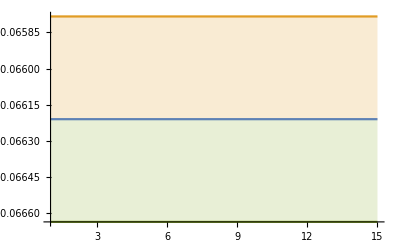

```mathematica
Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,15},Filling->{3->{1},2->{1}}]
```

```mathematica
SpoilHWFLOPlotN3=Show[Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,Length[meanErr2[[4]]]},Filling->{3->{1},2->{1}},PlotRange->{-.1,0}],ListPlot[{Table[{τSteps[[1,i]],meanErr2[[1,i]]},{i,1,Length[meanErr2[[1]]]}],Table[{τSteps[[2,i]],meanErr2[[2,i]]},{i,1,Length[meanErr2[[2]]]}],Table[{τSteps[[3,i]],meanErr2[[3,i]]},{i,1,Length[meanErr2[[3]]]}],Table[{τSteps[[4,i]],meanErr2[[4,i]]},{i,1,Length[meanErr2[[4]]]}],Table[{τSteps[[5,i]],meanErr2[[5,i]]},{i,1,Length[meanErr2[[5]]]}]},PlotRange->{-.03,-0.005},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]],markerlist[[4]],markerlist[[5]]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]},PlotStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau_{\\text{steps}}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3(\\text{NLO})",Magnification->1.2]]
```

-Graphics-

#### QCD mNLO - gauss

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={380,380,380,380,380};
NWalkers=200;
Nf4α1LoopBig={0.229421,0.229421,0.229421,0.229421,0.229421};
aList={1,2,3,4,5};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
csvData=Table[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"],{xx,1,Length[aList]}]
```

({mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.08126953162540156, -0.08377352424951477, -0.08006227931204632, -0.08097678519333608, -0.08923459763734543, -0.08831930827694189, -0.09093376465313505, -0.09253900537685664, -0.08447467309904164, -0.08696713433652485, -0.08474964780312816, -0.08560685278046333, -0.08716089249583239, -0.08914202298295, -0.08975057003010821, -0.0881209895705456, -0.08797160675769113, -0.09612344227863666, -0.10329405475950548, -0.09499249682374485, -0.1124045040349244, -0.1113316314295396, -0.09323636996930224, -0.09873435427118075, -0.10178022686395453, -0.10659394243439342, -0.10148451147729076, -0.10624690019811907, -0.09934943678296444, -0.09724522188328186, -0.10838188052112192, -0.1300736255955997, -0.1092375888312747, -0.09703599559929285, -0.09893216923554218, -0.09949241059723513, -0.10445834639335484, -0.21888186633934398, -0.23664911337962385, -0.11558218193483202, -0.11645861490784795, -0.11038215138678752, -0.09843159714337632, -0.09328769408053597, -0.0872934615894607, -0.08603985389267467, -0.08432423157390836, -0.08870713645235062, -0.08507118725422165, -0.08558532846085268, -0.08658326415544206, -0.08504782873117739, -0.0823308985539469, -0.0822222678852375, -0.08245637105562452, -0.08200733213557793, -0.08515387856944019, -0.08242358743637287, -0.08313785268551678, -0.08616628255218428, -0.08603283713965543, -0.08919879796070064, -0.10009324842830813, -0.09446740686877723, -0.09187324674644344, -0.09803132565176355, -0.08659175878349376, -0.08258021126881128, -0.0917391093681814, -0.10282314086222119, -0.08777495275457113, -0.08220949789823956, -0.0978902258517418, -0.08977101854739074, -0.08443109497292273, -0.08361720964909532, -0.09914206601789304, -0.09444526843339773, -0.08496155073195079, -0.08397647439900727, -0.08171383046701569, -0.08055318319095939, -0.08173708353826076, -0.08372599930786549, -0.08069803986590787, -0.08388239366100483, -0.0831350796025814, -0.08066598328843366, -0.07856616532437473, -0.08104541390116587, -0.08733661539098612, -0.08338873136255213, -0.08177388783276827, -0.08120923948037269, -0.08106695543955492, -0.08130335032799842, -0.0819625179473829, -0.07943140953084205, -0.07870590342026146, -0.08112235472639638, -0.0812425247901283, -0.08625244606601871, -0.0797276604027995, -0.0786631380065127, -0.07594080843127887, -0.07404804932488626, -0.07560608839784852, -0.07548221264712984, -0.07680894008712504, -0.07694116168888553, -0.07738321688129078, -0.07559885480133921, -0.07641233879397952, -0.07371942856629428, -0.07292497088636975, -0.07319222482382919, -0.07186271352357314, -0.07239700148369224, -0.07334268887194116, -0.07163990901763506, -0.07040645821538712, -0.07062657530186307, -0.07173511081571453, -0.07110618392628784, -0.07100870504219788, -0.0720161865782038, -0.07133088310692969, -0.07366148587382218, -0.07312292709641995, -0.07366910770914041, -0.0722076497132017, -0.0726054115523938, -0.07231709856073246, -0.07306382067311125, -0.0730752924539382, -0.0742294909451366, -0.07411234023413048, -0.07130043016972198, -0.07032176877274293, -0.07082216852048065, -0.07053299176163322, -0.07013428620248069, -0.06905309423559694, -0.06945995255060038, -0.07075289636900489, -0.07335057051425165, -0.0734461864344805, -0.08020434083968538, -0.07359286635237602, -0.0745955800517111, -0.0721731699560808, -0.0728878576091567, -0.07342005248184269, -0.07483455091030007, -0.07475449189798851, -0.0740557602710718, -0.07380718471249137, -0.07224427185863236, -0.0724727489945155, -0.07164587438349486, -0.07128978249767738, -0.07167724401811547, -0.07319335656627911, -0.07307906564343444, -0.07361597614687476, -0.07354229914475018, -0.07413456263945079, -0.0747915105869273, -0.07457861476995248, -0.07830676812616554, -0.09039577120397761, -0.08462198496652712, -0.08423595953112988, -0.08296721193998502, -0.08730655533277128, -0.0834108964892676, -0.08305540317290458, -0.08093265683951766, -0.07984956962794161, -0.0783211492351473, -0.0971810308346302, -0.08291853127273943, -0.08262819167748574, -0.08232522581022372, -0.08765631294254632, -0.08750310126811849, -0.08637281966995469, -0.08154208954137099, -0.08011390972171487, -0.08058696009768343, -0.09329007156287313, -0.07960014663551974, -0.0769129722625164, -0.07982876494603869, -0.07881499218810444, -0.07928142637193074, -0.08080490758351622, -0.0806011945900152, -0.08207578192898117, -0.07886953864320786, -0.07817589204401908, -0.07676303937805422, -0.07788481517106903, -0.07603673402327266, -0.07530252164583126, -0.07457435030676728, -0.07402902331003298, -0.0737390295846203, -0.07465917141456375, -0.0757171249592555, -0.07662357123725919, -0.07597995901802776, -0.07699341314322038, -0.07669672495617005, -0.07634401360744243, -0.075189735630612, -0.07639665530456402, -0.07498683863602287, -0.0746830334015467, -0.07460050570589438, -0.07395374949507402, -0.07428781703186166, -0.07428601124928508, -0.07437628422450195, -0.07592737200363306, -0.07618876251013422, -0.07905157315012473, -0.07999527602023335, -0.07996470411313526, -0.08511135818531075, -0.08312067295960829, -0.09201828448307446, -0.08479922549602531, -0.08020542529637514, -0.07627107537582208, -0.07696395354063919, -0.0803937270899797, -0.07961591599150922, -0.0794781144558775, -0.07895726901310897, -0.07676588945980156, -0.0772755838825066, -0.07664954142576745, -0.07646998262871561, -0.07545401698137431, -0.07783375162240834, -0.0762310285993586, -0.07643412979676432, -0.07708936023770238, -0.07733659687335147, -0.07738860571741724, -0.07909514058006042, -0.07886571258271671, -0.07834221037153902, -0.07810431009009042, -0.07664112588041248, -0.0763202281236186, -0.0760256193609853, -0.07820550157920071, -0.07779261454254159, -0.07871779214903768, -0.0803005796634817, -0.0791399679150966, -0.08027327098359745, -0.0808813187124428, -0.08076645300835997, -0.07982113663682876, -0.08185710429911527, -0.08202513267883835, -0.09029683869711413, -0.08935241329404413, -0.08852995231186346, -0.08806303052565122, -0.09391537186034107, -0.08821723574238204, -0.08394993323767846, -0.08134341360621382, -0.0824599379003402, -0.08860362173998025, -0.13296100891138424, -0.09877273870908804, -0.09424293157140247, -0.09812332400398072, -0.13724834246261355, -0.0969455375373043, -0.09291107741160476, -0.09358401337315811, -0.10256129772011642, -0.15317424637073163, -0.11984127057884568, -0.10314452160338151, -0.09690992046399324, -0.08981235585458545, -0.08912554039244903, -0.08691544008589924, -0.08395364084005963, -0.08245896389615921, -0.0838011901405706, -0.08362258698173658, -0.08348817722851627, -0.08385791297093181, -0.08474350795737354, -0.08155557476246701, -0.08338138597123633, -0.0862992178159412, -0.09113694441431212, -0.09134121147118528, -0.09618283184691215, -0.09549552273420213, -0.08923984050799172, -0.08847838344902342, -0.09196544557668143, -0.09360820728307107, -0.08983474316598061, -0.09800111990709796, -0.08805303174566939, -0.08459954319263972, -0.08295086803703189, -0.08111793387463863, -0.08196975334529394, -0.07947708363009272, -0.1635661215647057, -0.08215634041869525, -0.0818177324814113, -0.08090853646859068, -0.08016942318129594, -0.08204378227977513, -0.0844261090929655, -0.07964747862256533, -0.07945782048824065, -0.08315243918280917, -0.08429684212895164, -0.08125510069976942, -0.08248294450471297, -0.08653165474700983, -0.08632023023249563, -0.08279896370820955, -0.08488226862244468, -0.08385908606985203, -0.08175342711727196, -0.08138220704234117, -0.08427790486997377],[0.005432195783423355, 0.006736365347419175, 0.004590060861365994, 0.005370567576724942, 0.008452412409381216, 0.008075863999565435, 0.011020433029756, 0.0127305557781815, 0.00752857032817574, 0.008666630960873969, 0.00761944499427652, 0.00812762048817018, 0.008030194522676198, 0.0099519942851892, 0.009498028475176779, 0.00888872129529323, 0.008513700628367472, 0.013140730121536784, 0.017954208790703842, 0.011272107391198766, 0.027324374549828674, 0.02357658746649306, 0.010793915906616228, 0.013657822180864566, 0.016908736001204315, 0.017766388284426032, 0.01351964823795421, 0.01868497555196201, 0.015119137183153924, 0.013457172983106693, 0.01928958339624711, 0.03729383170464141, 0.023596082756024823, 0.01459292171337262, 0.015487719775124876, 0.015957085253338957, 0.018179538984689263, 0.10833529063079557, 0.11745417398660331, 0.023456755294457104, 0.023367181770301303, 0.019211164221221853, 0.011606899955237076, 0.009284342174852396, 0.0070476610825781485, 0.0058645146019734185, 0.005005705410212619, 0.006500039696942916, 0.004933850726983572, 0.00559940403511512, 0.005450612027461485, 0.005095151681773492, 0.004546632853759165, 0.004319010923555841, 0.004500055052936758, 0.003887909308198048, 0.0047388097531842754, 0.0037954530116004258, 0.003910367705447796, 0.0047336098837701245, 0.004531627642400617, 0.00650741965886944, 0.012196937704370504, 0.0077060922356610734, 0.007385095084757154, 0.012066734078766923, 0.006739882470625147, 0.005656065843588075, 0.01128861676063692, 0.023584925711932263, 0.009547665977982265, 0.00710492430191735, 0.020938906574508642, 0.010354162071826493, 0.0059825487214504244, 0.007336257608105249, 0.01602002267184717, 0.011162323646615986, 0.008353903477200676, 0.007945341136043055, 0.0067505825612992395, 0.005509538387559532, 0.005674087512778807, 0.005884506231971745, 0.0052121251556875095, 0.006753561899617097, 0.005441823348593283, 0.003425652035649052, 0.0029924279800430556, 0.003077928675448116, 0.006500191602056856, 0.0043440720088622825, 0.0037801223061046272, 0.0036779928379107084, 0.00458605935177846, 0.005250203150629365, 0.005188466328284048, 0.0041615237454834695, 0.0038045535150666603, 0.005515769568628984, 0.004589806704938634, 0.00801424546499671, 0.004278957491725582, 0.004739318755389626, 0.004360547275163172, 0.0037373718298535346, 0.004003046731723562, 0.0035458109383036235, 0.0037787109949654076, 0.003914364141138176, 0.0036927296998371705, 0.0034885778740264516, 0.0030794998619693885, 0.0027538970179493997, 0.002724560373266858, 0.0027032801143513936, 0.0029236244083571273, 0.0029300036589494064, 0.0032683185940098522, 0.0025454857580765305, 0.0029633239103139713, 0.0028440714257990246, 0.003005068657475633, 0.0025938846565995155, 0.0025707807383647833, 0.0035101195215870885, 0.0034362974716517923, 0.0054208326597252506, 0.004056228996501128, 0.004237616060059213, 0.003725929670900187, 0.0036490618486748655, 0.0035890122110064466, 0.003720305624206947, 0.0039074553926872575, 0.00415568002350808, 0.0038515569968647478, 0.003290905597619961, 0.003274069711912828, 0.0032154444440335678, 0.0029737983729422215, 0.002794907778861328, 0.00266253192711245, 0.003094408751925602, 0.0032370492795535397, 0.003678236428780154, 0.003221789974690723, 0.008698761743750172, 0.0026710324684018293, 0.0034390971057801176, 0.0019424735732349076, 0.0020706433113991452, 0.0019179155225403258, 0.0023215953025168628, 0.0025223325159438805, 0.002557468739848993, 0.0021561471159611575, 0.0021684568358284694, 0.002096191657896763, 0.0024173737273084903, 0.002290200980613951, 0.0023873342919922894, 0.003345649071362697, 0.002883455438195691, 0.0031722404966230433, 0.003293554672385459, 0.0038128758596800336, 0.004546272056745613, 0.004113316074133141, 0.005481999199586358, 0.013439840636050688, 0.008495639456109818, 0.008236110850227372, 0.006442766985950843, 0.009069641886344187, 0.008519880977813024, 0.007229895140933362, 0.006511773917098694, 0.005975167815034112, 0.00518836565118441, 0.01730546937849319, 0.007245528106395043, 0.007304549012602319, 0.007379754546278851, 0.009338109908219006, 0.00915556350124256, 0.008975371366412082, 0.005843543788063514, 0.0049278649031040365, 0.0056471310121721, 0.01815249294697788, 0.005330889875335065, 0.00405163455067057, 0.004638682290114378, 0.00475303422305359, 0.00505079715091285, 0.0067178291774983, 0.006014122122269143, 0.006244420811520567, 0.004459362895476104, 0.004586624538174537, 0.0037190141758173946, 0.003866426730127173, 0.0034204494030247974, 0.003747176233553122, 0.0024490074299175087, 0.0024880186868230384, 0.0024516916280887865, 0.0035648862759662062, 0.003412823717699419, 0.004068511051110562, 0.0034470360163165047, 0.003546400923851171, 0.0033099230232859125, 0.0030537505377311773, 0.0033055062834544493, 0.0030068598681050624, 0.00297167469834601, 0.0028929622130246546, 0.0031441756242748704, 0.0032589393162659307, 0.0033602020618307814, 0.003533493502000207, 0.003772628473862379, 0.004259839641167046, 0.004198568131383028, 0.0051312242613059, 0.005435112661744253, 0.005460566819519513, 0.00935366340480731, 0.007557510035742969, 0.01506999201405258, 0.008626061527378482, 0.006308298706491127, 0.004520917079997055, 0.004638120221941082, 0.005827806687903146, 0.005302084100944151, 0.005124668873635243, 0.0054380742060974215, 0.0036799835220970778, 0.003683634851795241, 0.003669520511107243, 0.003510005508850707, 0.003421017932297224, 0.0038355972706606975, 0.0035474232192033604, 0.003398194688050532, 0.003543089957914524, 0.0038381323527697953, 0.003851318222553217, 0.005030533616224089, 0.004419950191556142, 0.0038509083596737974, 0.003183399907344098, 0.003435420326837122, 0.003210601324028865, 0.0033461755334127435, 0.0042010389105992365, 0.003142573437907872, 0.0034861484044659383, 0.004060568032623269, 0.0040360217385968285, 0.0041878072103255165, 0.004235985803673478, 0.004679850625638237, 0.004490364213852088, 0.004738154980035912, 0.004795688181316564, 0.010268768960212268, 0.008165982623555721, 0.006271214214541689, 0.006310681276963352, 0.008111410917189713, 0.00584015673536031, 0.0051367614528971895, 0.004293689976864622, 0.004965400420477394, 0.008315178590772574, 0.04757707524515355, 0.013854087411513363, 0.009052824274832004, 0.011091017584992115, 0.0447428789925936, 0.010307570846138965, 0.007999228736137471, 0.009140293525065988, 0.01655349980551386, 0.06196341615766166, 0.03337805927383599, 0.018514716728254756, 0.01405109225050442, 0.008450723232699629, 0.006970555656455814, 0.004929866283979275, 0.003328600608000159, 0.0030449096425496903, 0.0035808691020256756, 0.00349419209688531, 0.0037284420775110035, 0.004394394662225963, 0.004996027801752017, 0.0045548803283811425, 0.005564607831048659, 0.006640613182977741, 0.007948732236873306, 0.008891110476758097, 0.009314127021493588, 0.009889653373212457, 0.00730691226654973, 0.006286117203903537, 0.0073018916922442485, 0.007742640714541167, 0.007634613773517748, 0.01457023929594301, 0.00785888778073865, 0.005399792081046722, 0.0044133306321645195, 0.00384907600252005, 0.003940998838519052, 0.004004324737352439, 0.09442715400164167, 0.006401265584391224, 0.00495904550336137, 0.0050658635473657555, 0.004779356490530741, 0.005162763618840661, 0.006788955463593627, 0.0052667003883394, 0.00571982927138816, 0.006685686639047822, 0.007588019446185355, 0.006094062331673237, 0.006944875869491319, 0.008512664573856007, 0.009484098103159236, 0.006728797062730973, 0.007314610871933942, 0.006179304788041484, 0.005410974378463668, 0.005288101699511482, 0.0059472458663256565],-0.073247,0.000554996,0.518884}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.04778433112290614, -0.04816170861642571, -0.048704674985585714, -0.048339671410150296, -0.048357227986726974, -0.04836232291963454, -0.047977208312128386, -0.0482626608323868, -0.048230658591463235, -0.04823003381165484, -0.04813098588718763, -0.048237435201525694, -0.048523135471057896, -0.04844307272685748, -0.04825853005112158, -0.04840685862699812, -0.04837089091508257, -0.04972562928137922, -0.04860712862513223, -0.0485870977420177, -0.048698711643435075, -0.048655216531239304, -0.04862700452656598, -0.048689590859375916, -0.04889584912196619, -0.04925725212890201, -0.049160965878359664, -0.04909166227801805, -0.04898637442975736, -0.048919129995316085, -0.04920846338329927, -0.04878676980408926, -0.048266096165877494, -0.048351382976472845, -0.04825547357950177, -0.04865527163069994, -0.04918120944019957, -0.049624715590735814, -0.04906105203353987, -0.04917383676824661, -0.0493508943134636, -0.04903786102288332, -0.048865497019138185, -0.04910574495811966, -0.04885292771754326, -0.04885947457572766, -0.048857369247726386, -0.048792175125383544, -0.049056331911974865, -0.049278590251855124, -0.0489732401461248, -0.048557323981331536, -0.0486115406513501, -0.04873050813743118, -0.04895576873168467, -0.049360933558752144, -0.04925679556424774, -0.04926720272310306, -0.04935603562017299, -0.04910534316858059, -0.04965810934238662, -0.049322991468810154, -0.04947238916834081, -0.049395601321242155, -0.049501212780319985, -0.049236500227501194, -0.04926019911279053, -0.04956514598606881, -0.049419557023413184, -0.049585650007161065, -0.050015857822742316, -0.04976344101716261, -0.04937986638221047, -0.049382997465987996, -0.049523822669384196, -0.049594585682708164, -0.049588810372069365, -0.04981655061054594, -0.049690924222784254, -0.04987589141265641, -0.0500578636625297, -0.05040017957673872, -0.050267542382793295, -0.05024363521928134, -0.05073231591473928, -0.05043490760795352, -0.049866352839691604, -0.05030241418063482, -0.05025795468431654, -0.049940972597354576, -0.0498513996477952, -0.049623226828006295, -0.05006170004313253, -0.05045335811796953, -0.050902945035948895, -0.0510787990084232, -0.05098288192396833, -0.05130334683302031, -0.051844824737712465, -0.05223061854644299, -0.052240829157694846, -0.052088976399593236, -0.05230346006653692, -0.05227496919214868, -0.05217204476633273, -0.05162324178923006, -0.05141490472547476, -0.05159855571270404, -0.05161672496891493, -0.05176291468338917, -0.0517912444978569, -0.05119938844984429, -0.05086985857579266, -0.050813588029969894, -0.051056410579166336, -0.05093142367043408, -0.05089592414148986, -0.05025234307361177, -0.05044372965412835, -0.05060054971247062, -0.05065211125062256, -0.05047304452377475, -0.05032321184193589, -0.05056571058639463, -0.050201266969392165, -0.050237573573466476, -0.05012792844538708, -0.05084206284403631, -0.053645067015263455, -0.07980477524871739, -0.059923330597419375, -0.05275714612532982, -0.053027723287156256, -0.051702169456471006, -0.051534531278399125, -0.05105585956294512, -0.05136338209975083, -0.05135402345006586, -0.051410817131291094, -0.051702660068560086, -0.05207394257050342, -0.052183366538104445, -0.05202539510628247, -0.05204654333356322, -0.05230134024881331, -0.05225675203950793, -0.052088815663984434, -0.0522097058880507, -0.05225782412159044, -0.052273654062024846, -0.05216857480184496, -0.052331718794342896, -0.05197683015836724, -0.05220850123408285, -0.05245376883910378, -0.05191400545685372, -0.05202237398445077, -0.05229347868983066, -0.0523340742540365, -0.05183576794526602, -0.05179422005858039, -0.051961845821513086, -0.05182530268452547, -0.05212286978768538, -0.05257402455098402, -0.05322747472824006, -0.05386296626006077, -0.053305773675823065, -0.052926345350981, -0.05373091683017001, -0.0543269181905633, -0.05525942382830451, -0.055264033703544005, -0.05478032010994382, -0.05573140128806235, -0.054784114753435, -0.05464832166606663, -0.0546290641312273, -0.055065411610993424, -0.06292725515044732, -0.06061817877622068, -0.05870018832956091, -0.05837947612813431, -0.056292130333441985, -0.05666520441734306, -0.056076572417644764, -0.05617282371489981, -0.05611677538899325, -0.05574422888853821, -0.05534830760280831, -0.055869550957534944, -0.05463645744802259, -0.055418134043874204, -0.0546739547246782, -0.054902466200567074, -0.054752078335692914, -0.054417555432974, -0.05470334478626764, -0.05382243429037903, -0.05499981398196336, -0.0547398035226769, -0.055413675529572014, -0.055999115002405626, -0.05507745329487879, -0.054341150962875416, -0.05394058946626581, -0.05441669512933618, -0.053616550062739916, -0.05405555512857751, -0.054131994011114876, -0.055741352425888326, -0.05858606250516163, -0.05778365056827098, -0.05718550970262726, -0.05841417872298794, -0.05702760627762493, -0.05911053990698592, -0.05734604427909886, -0.05949957273894318, -0.05843940810592788, -0.05747487523653892, -0.057761372561730244, -0.05682843716704407, -0.05763595385054886, -0.05664510716438449, -0.056541283408858806, -0.06364724842902235, -0.06046890861767638, -0.059040342171167076, -0.05975658828919802, -0.05737353847542141, -0.059822089690911, -0.06002543144448983, -0.06037709060959908, -0.06076377817734394, -0.05877523891960707, -0.061278229808078774, -0.06508764932856194, -0.07064376888142773, -0.06263385267125718, -0.06209004237684173, -0.06030598301613918, -0.0595943039370819, -0.05886707849048299, -0.05791984705552797, -0.05743789016551388, -0.05839734051675733, -0.0581398011732613, -0.06015387131804852, -0.06134289981239073, -0.05957813393945964, -0.06120100337241072, -0.05931130211436792, -0.06121161972145651, -0.061041301596907974, -0.061492616518602446, -0.060317820084848074, -0.060266016792543606, -0.05895745688926945, -0.0596527925884667, -0.059188073254831546, -0.05789505945734645, -0.05864085776565064, -0.06049388119015422, -0.060293279849126205, -0.059497402223047655, -0.05886296834765973, -0.060347988258675885, -0.059517472919283367, -0.06076287759065155, -0.06224725286254846, -0.062014727154051597, -0.06274561383447366, -0.06318714980413075, -0.06345514810439301, -0.06255224000227876, -0.06327796758740345, -0.06499968074910847, -0.06431021293407496, -0.06377437546855927, -0.06197486264969991, -0.06283444838919951, -0.06257052538272181, -0.0640052088203419, -0.0608839486839006, -0.06324169660015438, -0.06113185240376469, -0.06366643861595477, -0.06488640984891925, -0.06253149085175344, -0.06344015860502776, -0.06300929292869269, -0.06239564785414359, -0.06235653137013413, -0.06412206157621284, -0.06322816697906326, -0.06198614567492672, -0.06257023815311294, -0.06342238551685772, -0.06342004965920145, -0.06338835130232874, -0.064380188626429, -0.06469198870950546, -0.06523634312237943, -0.06485010375288869, -0.06605022687643053, -0.06494815658095146, -0.0626390601364621, -0.06263241909370458, -0.06263765643655173, -0.06371738731625065, -0.06356335240391003, -0.06246687590841895, -0.060876616545359724, -0.06093273932485897, -0.062433949688383984, -0.06293750159521082, -0.0631562077476491, -0.06325518575419935, -0.06749575368000418, -0.06794526458122599, -0.0644214516683698, -0.06334278006183965, -0.06289797299940154, -0.06258680343187231, -0.06291700215430333, -0.062312682797525686, -0.06247029995949191, -0.06328595438386328, -0.06365355156212313, -0.06398948108164149, -0.06478140431196126, -0.06542817584817162, -0.06601714894759148, -0.06540553945646517, -0.06746266376328008, -0.06632704228695953, -0.06444158449219523, -0.06638616390575089, -0.06811939659880817, -0.069643461985608, -0.06786766680345022],[0.0013221218896983873, 0.0014130417698381837, 0.0016379990017627351, 0.0014613431018897678, 0.0014547095704408332, 0.0014631886001218166, 0.0013326680854614543, 0.0014078665949824015, 0.0013846962199403898, 0.001379077789142985, 0.0013461643632065466, 0.0013462782154818609, 0.0014693357613242291, 0.001449988233822745, 0.0014282400026415058, 0.00156882335161155, 0.0016073520138028983, 0.002436231539738783, 0.0017007833379631108, 0.0017490490381485136, 0.0017662143110321643, 0.0017656214922646494, 0.0018047752326262694, 0.001709502432410733, 0.0018164898308399157, 0.001996099651974184, 0.0018773653734210994, 0.0017874476135684534, 0.0017652687197319782, 0.001773999866095732, 0.0019031832585421147, 0.0017338660879877043, 0.001594023762112883, 0.0016959057454585193, 0.0015689715935745569, 0.0017001580499143082, 0.0018652404323242996, 0.001965048600794951, 0.0016788383182815114, 0.0017123057888927254, 0.0016875791270468564, 0.0016152024620739926, 0.0015840792047001806, 0.001651843538785003, 0.001648476495641113, 0.0016311456151961348, 0.0017487681196013574, 0.0016919563744298104, 0.0017614010926505117, 0.0018085364656195413, 0.001601428106033917, 0.0014917606826633798, 0.0015276402367576229, 0.0015408038808595538, 0.0015747051389384595, 0.0016624749008736896, 0.0015778286124971976, 0.001625096546909071, 0.001582642471268977, 0.001520141204197181, 0.0016512950802567493, 0.001585115083339803, 0.001586753017913561, 0.0016376730058105357, 0.0015935693693767908, 0.0015012086963020939, 0.0015143676209819531, 0.0016220746733789145, 0.0016983842489476347, 0.0017068513084301494, 0.0017521093225113641, 0.0017095451587686506, 0.0015777771422672, 0.0016178193877671857, 0.0016768408823636257, 0.0017350001637478547, 0.001728525999703842, 0.0017933336516191758, 0.0017075444085767257, 0.0016895265515969758, 0.0016743933644824684, 0.0018092982421350802, 0.001805366603952132, 0.00170956838975314, 0.0019268463392635039, 0.0018366936967632063, 0.001617663178348687, 0.0017829429041143735, 0.0017264022396814675, 0.0015803539051677273, 0.0015298611052439763, 0.0015181830429399606, 0.00157107778447266, 0.001663537736353013, 0.0017003330701102239, 0.0016796865897333953, 0.001601182141307296, 0.0017199071902116708, 0.0018531461992202345, 0.0019188960657016494, 0.002018356033824437, 0.0020106747194870993, 0.0021392999174375234, 0.002071210458306411, 0.0020777376090357256, 0.002018209792885206, 0.0019235386214206216, 0.001985250383950624, 0.002033069048804186, 0.002188878113283883, 0.0022006628592407718, 0.001982640244594263, 0.0018192582519327575, 0.0017632431581779261, 0.001863237015121887, 0.0018295207130362822, 0.0017759411627518375, 0.001605496690084945, 0.0016774969512961793, 0.001782704904032159, 0.0017919878872371287, 0.001679767077042673, 0.0016043323484499488, 0.001719656788909429, 0.0015461971448989277, 0.001600577847097955, 0.0015263138180168316, 0.0018352356545377334, 0.004130209197471062, 0.029501804266096176, 0.009492420565293754, 0.0027682514867730535, 0.0028608518558362345, 0.0018867451410597672, 0.0016811378024305635, 0.0015233897741623907, 0.0015784792033490748, 0.0015654074633449358, 0.001552304298858628, 0.0015468484403258864, 0.0015996877696256109, 0.001675375642173176, 0.0016872655100649166, 0.0017025295174719242, 0.0017274961631216978, 0.0016185920052329695, 0.0015180902733102223, 0.0015718714895890345, 0.001607214623864987, 0.0015543528203608953, 0.0016277821289635334, 0.0015922750964061938, 0.0015560020785716675, 0.0016031609122983956, 0.0016419807355041317, 0.001538783532012755, 0.0015777007391534186, 0.0017230727963144024, 0.0017406009819025776, 0.001568452671725324, 0.001580170101808743, 0.0016166034878380435, 0.0016304394462245326, 0.001744390300705358, 0.0016591108869836205, 0.0018369466090556149, 0.0021837073337138205, 0.0019467101702818777, 0.001792079563852227, 0.0020651401898788588, 0.0022739595719130905, 0.002704876882176239, 0.002853536425799034, 0.0026426906424107106, 0.003069924650776252, 0.00242535492940503, 0.0022526467212261913, 0.002275844085666039, 0.002474024744027039, 0.008326487636534067, 0.005464246267465968, 0.003773511396392888, 0.004286079261611607, 0.0028769508100767484, 0.0032010333935063367, 0.002682416916200289, 0.0029226596829828194, 0.002787092335766905, 0.002661250223277994, 0.0024374410119845044, 0.002771275167108044, 0.0022708605772043112, 0.0025815548550137614, 0.002300750834482951, 0.002414220188015748, 0.0023057025811837675, 0.002121110146059841, 0.002229012026918072, 0.0020676847694997003, 0.0025420096031399148, 0.0024141209809665502, 0.0025654149591540394, 0.0029377525618185674, 0.002807403887841312, 0.0023891471440139348, 0.002319351931853938, 0.0024860741295221855, 0.0023874460100333905, 0.002475486907650059, 0.0025490966487660602, 0.003439387020516456, 0.005217030090420761, 0.004381997795658699, 0.0036288651542776894, 0.00429453681422712, 0.0035133799172160822, 0.004701370231986474, 0.0033484396604731067, 0.004095031556363764, 0.003508512156561147, 0.003208187198829071, 0.003317120797304645, 0.002988429050125687, 0.0032325421433850635, 0.002745488558192952, 0.002703860128972732, 0.00835454780530475, 0.005497686185887202, 0.0044703976038691865, 0.0047808871640156025, 0.00340042798405716, 0.0042988541469508685, 0.004270067854975585, 0.004613952577829162, 0.004806693007215502, 0.004220400040804519, 0.005736546363295028, 0.00839823905563991, 0.012687363265096223, 0.00626374949313727, 0.005617667049683637, 0.004554808288667054, 0.0043003078953770205, 0.0040680915469206, 0.0034496786274653296, 0.0031239541098078034, 0.003647586988456841, 0.0037508450870724365, 0.004937386431544022, 0.005210046143589139, 0.003913283807956462, 0.004707861869083487, 0.004170706927097263, 0.005286899295547695, 0.0052118492564183, 0.005773189113274993, 0.004973955442889848, 0.004172566171979317, 0.003575620612519794, 0.003989931505010665, 0.0034908350988030585, 0.002809944913067188, 0.002958992823487287, 0.003645289620446912, 0.003230730888180759, 0.002980829059555026, 0.002889061591657645, 0.003355624474337542, 0.0030645163913611134, 0.004028653050578264, 0.004209972771665829, 0.004296940610790503, 0.0049750772765542696, 0.004479590842810463, 0.004042517868659361, 0.003638439399095026, 0.0037920567765446925, 0.004768654884721748, 0.004447151550589171, 0.004307549949976848, 0.0033984050637867243, 0.003620869648755633, 0.0037914086353897725, 0.004407233875802157, 0.003244690222168331, 0.004115287600901639, 0.003424604694725518, 0.004188727638182882, 0.004527146810805397, 0.0037766573012289776, 0.00392482149663815, 0.0037266353333023725, 0.003742348177997486, 0.0036944171196199587, 0.004977937335926708, 0.004704196925868707, 0.004254546130266321, 0.004306512763309501, 0.004678428470156992, 0.004599773154320452, 0.004561020951641753, 0.004878612558160666, 0.004897945417453776, 0.004738739002012768, 0.004564545710670604, 0.005172355322173587, 0.0055934295532162415, 0.0041516101362956736, 0.004082306617392479, 0.003805982985055748, 0.00409581211025912, 0.00410199681132793, 0.0032526452802556045, 0.0028603966269415593, 0.00282433073895208, 0.003321217994684363, 0.0038164555133984217, 0.004143468998696857, 0.004308516426338662, 0.007950986330615159, 0.007737414229312336, 0.005007959029831332, 0.003827310936923293, 0.003471598420774911, 0.0031544460457944134, 0.003147277544107505, 0.003202723036540079, 0.0032720425570669396, 0.0036780581012857395, 0.003589717736655724, 0.0037581571793846523, 0.004062906657317591, 0.004449832871722014, 0.0052131408919140875, 0.004819601424965835, 0.005439463379839513, 0.0052632608644869365, 0.004251228247171089, 0.004627690566650478, 0.006437050352346661, 0.007131557202268073, 0.005602989592535865],-0.0469045,0.000720881,0.342591}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.03762590622897726, -0.037748422873361026, -0.037696234400433265, -0.03730567973373985, -0.03730210508868152, -0.0375252826213574, -0.03769351666882774, -0.03759591540308798, -0.03753984435331667, -0.03754584567275329, -0.03784786145097908, -0.03784701200696865, -0.03772964228779136, -0.037466561968165904, -0.037529495897458194, -0.03782688307372608, -0.03803609231849392, -0.038075703501787905, -0.03806791041740744, -0.037713442485092424, -0.0389701024847341, -0.0390037697076359, -0.039764805242184995, -0.03905684463291347, -0.039604015093949646, -0.03907700567218742, -0.039415378326730734, -0.03932530359019249, -0.039063516324605786, -0.03856779657589505, -0.03851664595324337, -0.038816082513780215, -0.0391016810812382, -0.03896145748433267, -0.03982856591594718, -0.039837940792614095, -0.04387346390260931, -0.041718562669266594, -0.04322902620621212, -0.04063884314773688, -0.040964733918190006, -0.04072023010743871, -0.04028268607470872, -0.040510806358801305, -0.041293137895134176, -0.040155503729733415, -0.04065801652131397, -0.04059444360725274, -0.04057575413828248, -0.04139128405498395, -0.04058323822884717, -0.040223985071308574, -0.04048736440823174, -0.040521414355324796, -0.04024811557646466, -0.04007369199858948, -0.039838457211705446, -0.039918342972676844, -0.040246939890263254, -0.04055789559403056, -0.04100200210720583, -0.04102541250381233, -0.04058614708497648, -0.04090681123886784, -0.04086917849710582, -0.04092063622998739, -0.040599283086691695, -0.0402955704025994, -0.040037863207154675, -0.04067657433601172, -0.04089369811655957, -0.04081096459932777, -0.04114379012703477, -0.04162969887614212, -0.042944573012092604, -0.04373413653717679, -0.04288495432124896, -0.04264049030178914, -0.042140851566844946, -0.04181558440109585, -0.04164820022559199, -0.042074744426356295, -0.04151118181589957, -0.04164581268253324, -0.04133771253642054, -0.04111090301477152, -0.04091067813943001, -0.041085736495126556, -0.04083732323493251, -0.04085595065057887, -0.040529821258898424, -0.0407452163955224, -0.041021589694582396, -0.041428575090458546, -0.04126361427757802, -0.041116778368772686, -0.04143972153621082, -0.04182960511653633, -0.042082403892630516, -0.042591656743997536, -0.04258611683354177, -0.042304841409143194, -0.04202711088335875, -0.042200534023210036, -0.04260778270575247, -0.041268620555240436, -0.04179583119921296, -0.04230467124068524, -0.043275642136920985, -0.04794777786689259, -0.055723193173672664, -0.06361350472161185, -0.044710869510389, -0.04316174217757238, -0.042239358201824735, -0.04164455443866251, -0.04203156724424018, -0.04126665260980025, -0.04124997698184976, -0.04095673084194339, -0.04077050040125163, -0.04066197919163084, -0.040653944525950364, -0.04086653222710699, -0.040698613685683706, -0.04063482363438147, -0.04060661584462623, -0.04087129513104347, -0.0411301577846464, -0.041488840968853344, -0.054915489671828514, -0.04496011452810393, -0.042126286401477864, -0.04708229386690143, -0.05870060460487798, -0.04352475466614817, -0.04241672662023552, -0.04145864273714324, -0.04100839991817193, -0.04117986077629606, -0.04172312449868208, -0.04215974747530368, -0.04209714277402036, -0.041951545101370606, -0.04251930407730669, -0.04265658575859955, -0.04327679016881647, -0.043251785976154, -0.04370450245383473, -0.04408491980847778, -0.04513324510731923, -0.04444329567337641, -0.044850271106812716, -0.04365318114927688, -0.04395482888139448, -0.04403365358236284, -0.04413423524616074, -0.04355598131671434, -0.04303271646162844, -0.042532588333591095, -0.04286508133144572, -0.0429839201855829, -0.04301201357323235, -0.042760376611430916, -0.043054115012030734, -0.043512509338068356, -0.0436499103110487, -0.043215342179216805, -0.04318619458391323, -0.0429494144973734, -0.04282727521336056, -0.0427383776488706, -0.042619371221012586, -0.04281230278114793, -0.04282487531007032, -0.042927950739520056, -0.04295983791655707, -0.0427256378608242, -0.04259834371979984, -0.043030842716024115, -0.04359753233500992, -0.04363488428187969, -0.04331383219107545, -0.0432493479723108, -0.043736895651064644, -0.04370971697590744, -0.044898544603666414, -0.04463918357838487, -0.04436394331491063, -0.04368488856082558, -0.0431041977400519, -0.04318190317114471, -0.04308631714731593, -0.04329154848863369, -0.04364553059805448, -0.04317646850069696, -0.04316410861526772, -0.0433716913010779, -0.043267796013997946, -0.04264887646792025, -0.04252399724928303, -0.0425159436306257, -0.04274386147934737, -0.04264361218488102, -0.04275315769226538, -0.04251837921240177, -0.04283738400212474, -0.042957739585671915, -0.042873604254588304, -0.0428196834760959, -0.042471382756131555, -0.04254795319650359, -0.04297136092143197, -0.04346759707443548, -0.043415831323553325, -0.042991075213836556, -0.043609693899824595, -0.04328464899884871, -0.043213813180035913, -0.04291425062289371, -0.04313105843897552, -0.04289093889797862, -0.0430232910976034, -0.04327193819590501, -0.04337953096950372, -0.043741947768452825, -0.04377326670004825, -0.044255663124932225, -0.04400783437328215, -0.04396066660483643, -0.04416481221033484, -0.04437282361439261, -0.04386574931086211, -0.04411014358459346, -0.044254383533708516, -0.04411213815831566, -0.043881737022176286, -0.04370213999503867, -0.043729188918109695, -0.04391963415060099, -0.04399369218281364, -0.04370098277577282, -0.04385205151619715, -0.04395817165163508, -0.043853500402960405, -0.043608341622085725, -0.04362929447940942, -0.043678970983688545, -0.043935149760040065, -0.044267118620007054, -0.044056782142885886, -0.04381490662194727, -0.043959369649927714, -0.04401022440160965, -0.043494201945596375, -0.043467246635860504, -0.043260907239525234, -0.04371861544344874, -0.04337119587914152, -0.04352531297914301, -0.04392708809864096, -0.043500518434352105, -0.04361912507032955, -0.04389655944611718, -0.04425704668770944, -0.044039974359382894, -0.04429750089815435, -0.04433026083569131, -0.044716517505202516, -0.04453157208900694, -0.04503944868266875, -0.04529949658835724, -0.04499803123197255, -0.04526426002935466, -0.04570558208882361, -0.04569961449224969, -0.04580077598391325, -0.04561849260917225, -0.04552664045394855, -0.046291916841188524, -0.04625661568834841, -0.04569659888131233, -0.04534321034740936, -0.04533557080460456, -0.04482427069931873, -0.04509752963281042, -0.045145427743802855, -0.04603815423457912, -0.04588681664567694, -0.04552338623114763, -0.04580800372167765, -0.046167980494488926, -0.04601224918132991, -0.04573102178881664, -0.04564146203076751, -0.04557413987798451, -0.045867943238501095, -0.045699051474850504, -0.04568882105238397, -0.045921019513168654, -0.04564354293749379, -0.04569788386263924, -0.045600998569294504, -0.04593883046911835, -0.04536999040523385, -0.045442286125738085, -0.04545780802435775, -0.04527725326835168, -0.04550143192876978, -0.04615831825552028, -0.04640249613866282, -0.04618211645412255, -0.046556284345954026, -0.04604250011580294, -0.04590168931180266, -0.046121636300498696, -0.04607011709416835, -0.046297565822312335, -0.04667618322998545, -0.04650102242914324, -0.04646841582527447, -0.04615797512973342, -0.04623485501656594, -0.04680304044463886, -0.04698512276284243, -0.04759054528978958, -0.04762558747510539, -0.048165885948880355, -0.04824082375541765, -0.04809025634587336, -0.04822748245174813, -0.048079659691459664, -0.04828128453923337, -0.04831057859689695, -0.04810538403452396, -0.04834759017389895, -0.04806851843963909, -0.04792423022378544, -0.04837682779849235, -0.048825840932132644, -0.04893554251889658, -0.04922948249594138],[0.0020470148454516312, 0.0020131155255672228, 0.0020042037164902504, 0.001839367808007344, 0.0018416387384448602, 0.001997797415259479, 0.0021458691470755066, 0.0020846455975844728, 0.002085645845791767, 0.0019929485144337344, 0.002198206343355878, 0.002124030413577188, 0.002141165848566444, 0.001996968503995003, 0.0019898710760015057, 0.0022493284092898183, 0.002320466209206017, 0.0024114128811123237, 0.0024503709724894487, 0.002287339211822134, 0.0030232191962615428, 0.002997663429194647, 0.003321663914201081, 0.0030028468190142956, 0.0033090820464193827, 0.0029462906697613265, 0.002965318266717131, 0.002931996053682948, 0.0028418322705930366, 0.0024453049808324965, 0.0024438854612332276, 0.0025650961595859445, 0.0029037893535455777, 0.0027927141343144636, 0.003560671902296642, 0.0035047093438706272, 0.0070975993909180345, 0.005014841014138267, 0.006393807973210803, 0.004164735893992821, 0.00429950238995297, 0.004045903053572697, 0.003518899113353874, 0.0035492371294114163, 0.0042315326626170754, 0.0033160940221939857, 0.00370914901471452, 0.0038376738155100057, 0.0036067237615702366, 0.004148650602629491, 0.003453338464012694, 0.003046579523374505, 0.002902278245767289, 0.0029648150309139858, 0.002926653565759065, 0.0027596184063447826, 0.002433232475375762, 0.0025693219410012737, 0.0027167751424987466, 0.0027671385806866556, 0.003051029991980552, 0.0031632319634420456, 0.0028008493265570416, 0.0029694487560895664, 0.002891475831215734, 0.002875823769680357, 0.0027679746473466354, 0.002623491322277375, 0.002544524012570628, 0.0029091706568478, 0.003025249099388569, 0.0029502277019946297, 0.0031696812858793247, 0.003501922232059566, 0.004407050372972771, 0.005215226499780359, 0.004379326803046894, 0.0042029222973976365, 0.0037977469048421767, 0.0034727200696013367, 0.0033455033270149846, 0.003466872536560184, 0.003080511087136738, 0.00318879594001564, 0.0028331050487950616, 0.0026186211917919246, 0.0025317194026954135, 0.0027946092654721044, 0.002620745269292489, 0.002598760135500771, 0.002439916669699379, 0.0024021892968654735, 0.0025324526032270396, 0.0026969900962029126, 0.0025917786748702195, 0.0024577303232389165, 0.002578320006527561, 0.0027986227244862845, 0.0028306705985560046, 0.002977371109263981, 0.003057770642037024, 0.0029669161101512115, 0.0029186107083104735, 0.0028815783977528616, 0.003218644547933334, 0.002529520589219406, 0.002749613702857541, 0.0030554577742696737, 0.0037485909364125586, 0.007732070417192536, 0.014936587422849928, 0.022813525714871843, 0.004777303118670824, 0.003626268081677024, 0.0030061632481367395, 0.002682892374659632, 0.002847664404602945, 0.0024300917976900925, 0.0024677044325180793, 0.0022914522995812515, 0.0021739939964245713, 0.002060081579092695, 0.0020671717782939606, 0.0021523118592650164, 0.0020578236675465053, 0.0020165815775524394, 0.0019655645397070824, 0.0020355439104394932, 0.002093595242523536, 0.002233904774702456, 0.014121148872853435, 0.004779935200017108, 0.0025547791775808806, 0.006525318960800616, 0.017264738988958157, 0.0033119278637317173, 0.002420200908022062, 0.002026827296819688, 0.0018252093000607308, 0.0018547971370398862, 0.0019577534805297813, 0.002114841086009045, 0.002055150617198193, 0.001958397377695225, 0.0022356572287758245, 0.0023109296191153993, 0.0025542985817320514, 0.0024991740460824645, 0.00291154181352923, 0.003225690355377314, 0.0043324195567638595, 0.00353774838503723, 0.004008840095867101, 0.0028308892696597317, 0.002836296594430457, 0.002925019733705995, 0.0028260302029037673, 0.002544896116703434, 0.0022427216625845285, 0.002070685911344811, 0.002096569465732744, 0.002139806784867766, 0.0020162609423903096, 0.0019785227446292783, 0.002026138618170874, 0.0021210091709439024, 0.0020861701149749302, 0.002008097393322132, 0.0019448317698690844, 0.001871584458263006, 0.0018276367888417752, 0.0018138156055689456, 0.0018882242643013599, 0.0018847471500815364, 0.0018869169353116497, 0.0018423935769188206, 0.0019436359687262982, 0.001873453660259391, 0.0018076803094829025, 0.0018903841236987864, 0.0021127790334907067, 0.0021911581801322658, 0.0021502488258760785, 0.0020995346664864816, 0.002290960972142735, 0.002355242615679963, 0.0030090252188468905, 0.0028838167747619833, 0.002770242531926516, 0.002260626271753442, 0.001995310256375202, 0.0019775415553165013, 0.0019717041822229055, 0.0020510365184398262, 0.002095630679300612, 0.0019225234068189427, 0.001841497091047017, 0.001863608151746623, 0.0019184081731048559, 0.001652930464764071, 0.0015849966159803988, 0.0016240320991201315, 0.0016441854650999376, 0.0016546448943528067, 0.0016901197082015832, 0.0016044007268437948, 0.0016626134817335236, 0.0017041899993426955, 0.0017049531936489907, 0.0017166168496179877, 0.0015988904226339876, 0.001670872554838956, 0.0018101965011814041, 0.002028521246939284, 0.0018845702671103982, 0.0017174626409653083, 0.0018908800269758672, 0.0018016727398576888, 0.0017514389166156086, 0.0016022493376674277, 0.0017098250867621787, 0.0016397457167015377, 0.0017150362262036904, 0.0017800389246961476, 0.0018498938769550934, 0.002095915982493473, 0.0020091810224462194, 0.002229898970585166, 0.0020503189325135128, 0.002087325726259887, 0.0022328160645192466, 0.002286351682130455, 0.0020580484463793704, 0.002095125260386203, 0.002137501171290264, 0.002201983978482285, 0.0021147226459104986, 0.0020793419323222894, 0.0020805725626980237, 0.0021033483963628016, 0.002089434862876119, 0.002013508010316373, 0.002236686203315765, 0.0020936389962601786, 0.002073949019083646, 0.0019252969157078567, 0.0020002398251465327, 0.0019764742448684248, 0.00215663820281828, 0.0022801134189883105, 0.0023024431725104937, 0.002062013030042379, 0.0020852658060728523, 0.0020314038458603577, 0.0018028423859534626, 0.0018031946831306364, 0.00179215240180107, 0.001895828593592391, 0.0018269172958863644, 0.0018522984754768893, 0.0019030853420574226, 0.0017325720758286998, 0.0017835268370547518, 0.001786391702359595, 0.0018089573728446208, 0.0017506259880675046, 0.0018201856968889914, 0.001803971890694424, 0.001927131327722724, 0.00189897548732737, 0.002014752871126175, 0.002010811419022875, 0.0019139242829560891, 0.0018916404444717962, 0.002017356588472954, 0.00206646998549672, 0.0020237359816512646, 0.002037970742468664, 0.001961777928828456, 0.002161381397268084, 0.002119621837100949, 0.002010796663358064, 0.0019549954089269983, 0.001987556873058063, 0.0019500056810407434, 0.0020370625768182074, 0.00206502380044228, 0.0023424752619018037, 0.0022450519528146983, 0.002157712104556776, 0.002239098898463587, 0.0023822421020998903, 0.002370120135802241, 0.002281392844091475, 0.0022746089257910753, 0.0022900233863698337, 0.002393573835801988, 0.0023661035904971586, 0.0022785914603541146, 0.0024375429636439992, 0.0022903595973157824, 0.002359604336652975, 0.0023193955648411783, 0.0024264481710798472, 0.002192284489648679, 0.0021895315899611387, 0.0021873672650222125, 0.002162767083939156, 0.002322189454809563, 0.002481560413179588, 0.0024838662971708157, 0.002284971640981413, 0.0024157983964835815, 0.0022837125142557194, 0.002283384003858441, 0.0022616524195233512, 0.002236136217270532, 0.0021790895900989297, 0.0022985195370092667, 0.002347110952517929, 0.002294792248258493, 0.0022178530940193957, 0.0022781430419977727, 0.0024993032240283888, 0.0025377981930826115, 0.0026920401356571606, 0.0026552378543479803, 0.002888013317582607, 0.0028450082487825783, 0.002697122157068759, 0.0028578909126276276, 0.002670750120215011, 0.0027679591485021355, 0.002758718514840818, 0.0026140068702553065, 0.002697395598196326, 0.0025920864380474897, 0.0024991921760896614, 0.0025460765664271057, 0.002725095394145212, 0.0027403559392211677, 0.0028050065523131853],-0.0372531,0.000732001,0.208069}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.028530019393609985, -0.02843618130980591, -0.028472134303686353, -0.0285861159559755, -0.028384988555161732, -0.028349317025666627, -0.028570168188864348, -0.028500002849998866, -0.028624851720550414, -0.028519751042239458, -0.028500874925887824, -0.02851244330520562, -0.028522454210702937, -0.028564686449040963, -0.02858051741743094, -0.02857911095261639, -0.028550906862666446, -0.02865592302815167, -0.028649956902451784, -0.028632820318454915, -0.028729878670107605, -0.028726398316780737, -0.028800466908178522, -0.02889968753959778, -0.028827144338878688, -0.02870480048511568, -0.028716307539350477, -0.028649626890981397, -0.028627097637942536, -0.0285476960705309, -0.02847888392933361, -0.028491069328742936, -0.028371115092745185, -0.028351920608364622, -0.028334580480675563, -0.028361382163602105, -0.02843682162250713, -0.028498737512074695, -0.028490702737070203, -0.028433521239450168, -0.02847513341720042, -0.028543853666002386, -0.028585838248173148, -0.028646558716535986, -0.028644856616330237, -0.02850783943532923, -0.02847914574297934, -0.028473156320577796, -0.02859507176843156, -0.028630528986047652, -0.028722750453461322, -0.028655170964292258, -0.028818572094444828, -0.028828842906637744, -0.02878064906357841, -0.028676100690216866, -0.028577365160621003, -0.028656451111793324, -0.028709112811246235, -0.02885498555487821, -0.028914381975157968, -0.0288998855051987, -0.028979854814581842, -0.029015328326146658, -0.02903362667926278, -0.029032711679742047, -0.02904753378432829, -0.029107245514378766, -0.02914976271782888, -0.02910672530466155, -0.02915424757869664, -0.02912889920551466, -0.0291357522138528, -0.029204997477939348, -0.02926934258958811, -0.029262192544295153, -0.029388144697135944, -0.029379207291173947, -0.029263667298991245, -0.02919113070729211, -0.029287826987605348, -0.029349440494638702, -0.029345359507503017, -0.02928192198954261, -0.029304261396444743, -0.029199495754016647, -0.029150393595670746, -0.02906956648970856, -0.02903518102405527, -0.02902227712651513, -0.029025789624766606, -0.029102968568651032, -0.02929681721409848, -0.029348022435659822, -0.02938819064708745, -0.02954112831958691, -0.02960338479267208, -0.029623854876498462, -0.029820324868817083, -0.03007883408154447, -0.02995743916201628, -0.029833413168077867, -0.029785286330706453, -0.029943251303317014, -0.030163022176010797, -0.029896645007691538, -0.029881717158394102, -0.02979530398299514, -0.029700359455904043, -0.029838460971259542, -0.029944718519960348, -0.030153725349465525, -0.030554135120171473, -0.030211509040946993, -0.030499125483570467, -0.03054079969690385, -0.031376353771424254, -0.03199516375997905, -0.03089299350936286, -0.030633435096275096, -0.030467092244687403, -0.03017142959177421, -0.030206571859483965, -0.03008410698386796, -0.03016830727966844, -0.03029840300074641, -0.03013891899066101, -0.030231882548125, -0.03022077252199628, -0.030203880247831084, -0.030284650982061304, -0.030267561256555196, -0.030262354498169896, -0.030517766804646896, -0.030624252779969607, -0.030643019269236696, -0.030669296430794003, -0.030614276417148856, -0.030409760019058447, -0.030424418004456607, -0.030733167169161406, -0.030728200763245603, -0.03090969258335962, -0.031175002960944366, -0.03122097115122628, -0.03121435201367269, -0.031170092608822447, -0.031402791473177497, -0.031728561530657916, -0.03155871775737899, -0.031587623345361956, -0.03159562979866017, -0.03176642765498932, -0.031798668660062354, -0.031753491791262176, -0.03175974609301583, -0.03196889189937951, -0.031855589843099476, -0.03201601378658796, -0.03196868784184305, -0.032092915427237315, -0.03187798946757177, -0.03215140897062609, -0.032048489721802534, -0.031870036630025605, -0.032135948946452664, -0.03220092544658846, -0.032037030196609945, -0.031916858881228784, -0.03209738787469355, -0.03222010066020359, -0.032242417411695264, -0.03227756607270893, -0.03243525428249551, -0.03286586575805583, -0.03270792199488197, -0.03253443089697181, -0.03221825219801436, -0.03223850100142731, -0.03260319696047001, -0.03234236658093925, -0.03243572343998331, -0.03256133004291817, -0.03253205320249433, -0.03270998535140361, -0.03293510604979214, -0.033100824362900384, -0.033008087930692716, -0.033177727024436145, -0.03352485482320985, -0.032990986319639294, -0.032732862417030155, -0.032783522779065224, -0.03325400101459344, -0.0334153711854475, -0.033608314901578604, -0.034575019513731105, -0.03523016412334097, -0.034423775978687385, -0.03476397901982357, -0.03593798156327333, -0.03626495812607366, -0.034988262044604604, -0.03504948457443276, -0.035522392205929336, -0.036258453605205306, -0.03614775534644794, -0.035416900896057216, -0.036020509354672915, -0.03499339848871069, -0.03465489166278431, -0.034772195711423586, -0.03530522570861325, -0.03553584122103843, -0.035467144827972225, -0.03526128939049571, -0.035686767877247845, -0.03521244399262583, -0.03659656278680007, -0.03635900712823529, -0.036285843942178965, -0.037952706003517196, -0.03844408352853849, -0.038402028693326436, -0.043707838599075455, -0.04122723052541798, -0.04092218773922391, -0.037961851035718204, -0.037589610191089626, -0.0365912181997449, -0.03679312365229449, -0.03732599356527324, -0.0374628503946082, -0.03682263292503578, -0.036179413709375774, -0.03557027153106019, -0.035156520460618526, -0.03477091831609912, -0.034513467989710764, -0.034938980559524914, -0.035403701494649296, -0.03537471392816933, -0.03557133582173576, -0.0350943558272995, -0.03551166789261321, -0.035678908928122054, -0.035760889391823134, -0.03595295174866048, -0.03574154344095966, -0.03585504520996453, -0.03579814531624422, -0.0358860723792977, -0.036379064076977816, -0.035335951643619294, -0.035016596949374625, -0.03507508659656393, -0.03495613650285066, -0.03568354815600548, -0.035764135344316536, -0.03592667362872646, -0.03551406820507997, -0.03532303640039672, -0.035695824558737745, -0.0365111034269064, -0.03642148309058319, -0.03665527939201807, -0.03681844986220329, -0.0368304037010569, -0.03757959314905859, -0.03752253658969661, -0.037796341694515935, -0.03806641010458709, -0.03794547166812023, -0.03824052163739559, -0.03816667316079848, -0.03743774327345674, -0.03762772970959313, -0.03808432122003004, -0.037403470364211384, -0.03730590548567015, -0.03729377051154235, -0.03722986893685032, -0.03678810126888815, -0.036492033811598795, -0.036088266737743784, -0.03661118157906479, -0.036476062109187884, -0.036544843466135124, -0.03655362280491845, -0.03688884014943446, -0.036973325436541346, -0.03716100107089135, -0.03710112182803352, -0.03741514493037545, -0.03755019844708378, -0.03722473525625039, -0.03742834153690411, -0.03768648899037634, -0.03760298937104704, -0.037266009957063966, -0.03697593751377245, -0.0368508096152988, -0.036968795547120264, -0.03682466800267789, -0.036908488799849655, -0.037013286523222735, -0.03666830857555007, -0.03677590642190135, -0.03671969217026554, -0.03690586822541727, -0.03709919850715534, -0.037334494229070744, -0.0376247049028358, -0.03777374043565159, -0.03773872184139473, -0.03772146345150717, -0.03701390950448708, -0.037626163031370015, -0.037674685737222345, -0.03787966102360793, -0.03815442872770535, -0.03825749417188376, -0.03796983150175466, -0.03786252066521624, -0.03783410060229709, -0.03789031871032483, -0.03836576786357934, -0.038560871825501636, -0.03828583712183186, -0.0386448254272266, -0.03845331497624136, -0.03870310365837826, -0.03859734908265975, -0.03818029413856801, -0.03799532154976245, -0.03812751823272516, -0.03769456393668155, -0.03788093890448597, -0.038374277252875726, -0.038499346492181924, -0.03923955868732856, -0.039627835715046994],[0.0010779780824999828, 0.0010119759596332717, 0.001033731197654029, 0.00104164716217662, 0.0009660325984358742, 0.0009577074236285986, 0.0010360106577934351, 0.000993200313521728, 0.00101057028392485, 0.000985606008022766, 0.0009579095960171229, 0.0009614369878861455, 0.0009525326426046948, 0.000979740826463321, 0.0009912020494408623, 0.0009809944951467075, 0.000985506232262381, 0.0010001494807905219, 0.0010095595192103537, 0.0009799884994802774, 0.0009943282841836391, 0.0010036001653224297, 0.001037221702872955, 0.0010560310642774818, 0.0010588209160905019, 0.0010222437249426876, 0.001021527037310512, 0.0009921829458716756, 0.000974662782791168, 0.0009506864489184117, 0.0009416371992710834, 0.000936226285374823, 0.0008971961594455468, 0.000905027829216598, 0.0008925852508408843, 0.0008905562879888757, 0.0009013520617426384, 0.0009188308445646583, 0.000930452309811486, 0.0009064016115262441, 0.0009093548461040202, 0.0009404961386105546, 0.0009417199540940228, 0.0009530984813153474, 0.0009629104525084234, 0.0009292555896233966, 0.0009302733998232351, 0.000925645461845362, 0.0009565415624618489, 0.0009530752033237624, 0.0009699797482600667, 0.000940422743725827, 0.0009811327573530223, 0.0009707315327757171, 0.0009655945376313258, 0.0009287697999870279, 0.0009022061895230962, 0.0009266197633291684, 0.0009417821732364357, 0.0009791755050967297, 0.0009998115489655648, 0.000994875013112681, 0.0010225389245286211, 0.0010567539672954726, 0.0010537431336226234, 0.0010525701811447562, 0.0010650942757894828, 0.0010738111510739203, 0.0011060804745139405, 0.001066150303574719, 0.0010890722069250769, 0.0010344236441155775, 0.0010279277057225814, 0.0010496030387034782, 0.001062784046833578, 0.0010568748584468292, 0.0011311024160694735, 0.0011228813920806575, 0.0010738729125323748, 0.0010555560293370508, 0.0010804494842546319, 0.0010791644160299217, 0.0010612900465283733, 0.0010085332449135378, 0.0010184090021048105, 0.0009849407084724108, 0.0009895305849844593, 0.000976899903465983, 0.0009605310171460232, 0.0009305159167856888, 0.0009167715764721825, 0.0009283474612688304, 0.0009686194935938802, 0.0009734223830780263, 0.0009678682107707642, 0.0010134807490131343, 0.001023520934419198, 0.0010463632761533298, 0.0010945444144348886, 0.0011678684234580686, 0.0011481119069315525, 0.0010652330427635799, 0.0010577763521254111, 0.0010914433650835878, 0.001172358847566992, 0.0010886681792791324, 0.001065169781395939, 0.0010331933102372818, 0.00100585985467548, 0.0010520818424403797, 0.0010705204696773057, 0.001172285424200761, 0.0014445765185751897, 0.0012139614339771673, 0.0013728165385917068, 0.0013836358884404692, 0.0020115960190124544, 0.002463865876676586, 0.0015666621050383486, 0.001369551506918987, 0.0012910831163390586, 0.00113211988898256, 0.0011536594652601405, 0.001072203927446709, 0.0010856288377361608, 0.0011536357168025295, 0.0010776318776281105, 0.0011021432700899219, 0.0010705480714404405, 0.0010389724563374348, 0.0010550827152724916, 0.0010337291367804884, 0.0010279218117514076, 0.0010889197612661582, 0.001102432438155098, 0.0011079058682381326, 0.001111806386573851, 0.0010955967472166253, 0.00104956553959853, 0.0010329274945019185, 0.0011480752388947678, 0.0011338906953333038, 0.0011861339881041617, 0.0013106822827302375, 0.0013084394119201141, 0.0013038494884462157, 0.0012636318693440543, 0.0013489883184648005, 0.0015192730146816678, 0.0014224813197342486, 0.0014319896337193097, 0.0013700026247724481, 0.001457038296009811, 0.00143468279995356, 0.0013898795501308717, 0.0014016031263058561, 0.001513372569299991, 0.001411766412672769, 0.0014422660740588608, 0.0014304518568917, 0.001465605681280353, 0.0013907768524523548, 0.0015217224181416546, 0.0014869285297422277, 0.0014007637316250728, 0.0014913964224542004, 0.0014797792915819486, 0.0014254684818101105, 0.001378843169269628, 0.0014259353069974274, 0.0014463434286716972, 0.001405916305803187, 0.0014589151324061217, 0.0015416695961107073, 0.0016794244484184496, 0.0016285825585973435, 0.0015243215592368798, 0.0014262772247299901, 0.0014388755564277802, 0.0016001941324460859, 0.0015161558907645725, 0.0015320487271702039, 0.0015828785186868721, 0.00155272883745653, 0.0016751188982484656, 0.0018013552244213122, 0.0018923837462536896, 0.0018457930143199468, 0.0019173326433910276, 0.002066576046496959, 0.0018166325217120563, 0.0017286449590425935, 0.0017867846708319915, 0.0020618511376141414, 0.0020503178148796697, 0.002211596100915292, 0.0027545603658305005, 0.0032429377883279073, 0.0027359258711794386, 0.002934825219209004, 0.0035940393680096426, 0.0038575469219847077, 0.002932790136567492, 0.0029826377939556376, 0.003306343267997045, 0.0037590785627761645, 0.003809851001539064, 0.003348870083808314, 0.00381003426742921, 0.0030438559809880857, 0.0028059402235620064, 0.0029403627356967307, 0.0032325919649247377, 0.0034675612278146327, 0.0034530905731380984, 0.003237512943134805, 0.003519145617764793, 0.0030707878123145734, 0.0039466616427360135, 0.0037014122272186504, 0.003587825672854972, 0.0048264778174072105, 0.004899768130944468, 0.0048375028895325115, 0.009037190010301382, 0.006956796218465528, 0.006804730148997718, 0.004713649208879262, 0.0042835344442609564, 0.0036128793691259445, 0.003697915389068467, 0.004058465197438449, 0.004100679590347814, 0.003599400102157612, 0.0031777971150364157, 0.0028985202948205494, 0.00263752348113836, 0.002475758511424174, 0.0023416476168779464, 0.002490865736986576, 0.00265852731521012, 0.0026377265863284953, 0.002824186329586152, 0.0025379865090820685, 0.0028862674388081093, 0.002969632870257264, 0.002952376412152932, 0.003054562622045678, 0.0028912047159431057, 0.0029304074430756472, 0.0029329245610223414, 0.0028958066339659226, 0.0031375658956750646, 0.002560803477008089, 0.0023923667693959753, 0.002406854205216365, 0.0024047615837817942, 0.002695695154240214, 0.0027967853955988787, 0.0027362457213337063, 0.002431166782713171, 0.002423116171776124, 0.0026063760918327915, 0.0029289383214418188, 0.0027885444703586036, 0.0029023979259879843, 0.0030704328869707777, 0.0030129665262453326, 0.0033999473379975357, 0.00339302431798788, 0.0033998715908331216, 0.0034714818327214176, 0.003413239547070395, 0.003528942334865168, 0.003419037877518601, 0.003085662938595402, 0.0031998298355478505, 0.0034927376138144377, 0.0031417127963389332, 0.0031380956686857127, 0.0031410801187617718, 0.003181493436559634, 0.002923414174716298, 0.0027335373964920803, 0.0024508637199103863, 0.002610665122669818, 0.0025736963927869808, 0.00262363391646037, 0.0026020909766170533, 0.002755889877771466, 0.0027317562156440596, 0.002838110008185802, 0.0027967281959643247, 0.0029611640604374303, 0.00295550621816855, 0.0028539830972524895, 0.0028698524116702448, 0.002865717314295238, 0.0027742017352355665, 0.0025905756178519154, 0.0024926581983183344, 0.002453280481770516, 0.0024895848462796657, 0.002361266244801071, 0.0024285372437989248, 0.002467267257480038, 0.0023169150255108236, 0.002395261657718835, 0.0023279580398719315, 0.0024009400035646233, 0.002518137984604674, 0.002570023050682309, 0.002624256635057862, 0.002698789039649881, 0.0027059704231205185, 0.0026382002594093072, 0.002375593376010044, 0.002633890229710226, 0.0025894193431964772, 0.0026461413547345033, 0.0026786688354828356, 0.0028004723356112827, 0.0027223313594631174, 0.002641082345567987, 0.002659167425248462, 0.002670408604040076, 0.002857006865528974, 0.0028206619921236466, 0.002787683729384481, 0.0028671889942448454, 0.0028199299119581298, 0.0029338476476726636, 0.002840290399380418, 0.002723606950445387, 0.002590777462265273, 0.0026170187128203154, 0.0025441891497726492, 0.0025387379001835047, 0.0027849535091031023, 0.002879989960663495, 0.003194618272345186, 0.003376670966472961],-0.0274208,0.000590472,0.186017}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.02296184995401622, -0.02297661335102645, -0.023002802912515496, -0.023025492564407463, -0.023051416004230323, -0.023069106402849964, -0.02312542618262598, -0.023134525910045167, -0.023167742597413696, -0.023147316744709635, -0.02318074946817309, -0.02322013772619449, -0.02318349194261683, -0.02320534536236704, -0.02321892030081499, -0.023249547981367583, -0.023295373912178032, -0.023275730097441338, -0.02324602819707591, -0.02323331485424599, -0.02326206193832697, -0.0232246204478713, -0.023268727701378913, -0.023274531836047763, -0.02327760758123921, -0.023305509858482298, -0.02334158207218564, -0.023357161806762988, -0.02336129300004313, -0.02331974559742225, -0.023318251722156604, -0.02330977602442356, -0.023277823285162386, -0.023229031760239712, -0.023213795360937584, -0.023205877219557663, -0.023240502936141844, -0.02329553250616911, -0.023314494531815298, -0.023278385449767437, -0.023331604666374496, -0.02333796610288218, -0.023344600649261762, -0.0233649598295129, -0.023356080060895075, -0.02334816481102389, -0.02336069010494513, -0.023350879993857515, -0.023408422505006004, -0.02344568835708626, -0.023443009174340456, -0.02340463388525355, -0.023492179670251065, -0.023482391998685438, -0.023537040930470095, -0.023527357547898496, -0.02355679100508625, -0.023674165090517577, -0.02371138614689562, -0.023740883564926457, -0.02381186448036597, -0.023796160055097125, -0.023808596888591205, -0.02378421422446124, -0.02381530193502111, -0.023861976290199493, -0.023829836928157672, -0.023897662488695112, -0.023889987774287514, -0.023893677103421725, -0.023969601212036656, -0.024037427510931096, -0.024038541354167543, -0.024081916560643946, -0.024137959060359922, -0.024118387582579646, -0.02415937008421685, -0.024108090294590052, -0.024128006635660778, -0.024137312489115385, -0.024176317774094444, -0.024210598104267966, -0.0242261440993613, -0.024295761197334214, -0.02433061491113012, -0.02422860872358896, -0.024219659945460655, -0.024198616219230088, -0.024251492158137714, -0.024167436211383387, -0.024196489677719913, -0.024239232273679873, -0.024271900303465814, -0.024305616881627697, -0.024371755802346618, -0.024475245282252162, -0.024650565070917896, -0.02459605367082448, -0.024658047875482498, -0.024731877559643605, -0.02473542498020775, -0.024737276237458347, -0.024657794367901265, -0.024831825530998847, -0.024943351870275965, -0.02487160764228773, -0.024801083590308668, -0.024761233604865818, -0.024700110132828582, -0.02465891541239069, -0.024696587476753552, -0.02472209726763863, -0.024803304522904072, -0.024826453132914525, -0.02491723045091881, -0.024908790889984142, -0.024984162208498563, -0.024967694253339428, -0.024968483245131803, -0.02508632505493447, -0.0251198759808258, -0.025157742625797803, -0.025291335396207523, -0.025122110503641968, -0.02514040152126656, -0.025015870049968473, -0.02506650927024475, -0.0251731455374306, -0.02512253452167755, -0.025121781408096927, -0.025048617556016634, -0.024973515817392787, -0.02507321202119641, -0.02503255572568298, -0.02503280819178466, -0.0249638324968709, -0.02502753537197445, -0.024858924547280583, -0.024894115341737216, -0.025049248277809404, -0.024918670939339128, -0.02494072938849451, -0.024956810825609608, -0.024931739512356013, -0.025025246441449815, -0.025308562364666744, -0.02535068257014344, -0.02534359860530763, -0.025336452299713392, -0.025284414230827827, -0.025164305134742958, -0.02508321743283348, -0.025004609921948813, -0.025151945356820384, -0.02511845324744889, -0.025211791660016983, -0.025342541760240964, -0.025306368348346518, -0.025486459732116995, -0.025547060393628564, -0.025357951233050468, -0.02525151622812263, -0.025188634764383426, -0.025193152890362502, -0.025186488807225203, -0.025349428962323124, -0.025332101080739557, -0.02529517329057285, -0.025245203935820512, -0.025276816603858124, -0.025190428713469097, -0.025274908159975035, -0.025300340566943698, -0.02520308074077418, -0.02514171368540339, -0.025157892441199703, -0.02520454152020825, -0.025214802486524572, -0.025119842867773075, -0.02516455165187097, -0.02509685267992984, -0.02516724711781054, -0.0252408968812412, -0.025271751611822556, -0.025228845063339497, -0.025219797465112905, -0.025213613829111744, -0.025211787749181928, -0.02523993074880002, -0.025300872222465316, -0.025300535991976604, -0.02520978588181303, -0.025166157954087772, -0.025082535182432267, -0.025200849569196646, -0.02521758470137096, -0.025362695917202506, -0.025416749274508158, -0.02528140231157454, -0.02529100605495357, -0.025358047882068493, -0.025438828078572805, -0.02535879288469341, -0.025348448821995277, -0.025378825262962593, -0.025259440281423576, -0.025310296253465443, -0.02540119442644592, -0.025393554288731517, -0.025422061245484913, -0.025399670563145956, -0.025350550316289508, -0.02542145247306379, -0.025416324532152118, -0.02542214172451208, -0.02541982962048864, -0.025452500450013283, -0.025546137696597665, -0.02556748062347533, -0.025551314414716354, -0.025594937352045228, -0.025466828933057534, -0.025473260071943612, -0.025447743222954962, -0.025537298172196545, -0.025609937118693454, -0.025705556140330064, -0.02570487077212733, -0.025645236154450603, -0.025658663755193066, -0.025643639428099062, -0.0256375411064745, -0.025575206040456815, -0.025613712487143662, -0.025630296255326583, -0.025484627011873626, -0.025449400811044878, -0.02548201234364203, -0.025526770975664106, -0.025614956847205512, -0.025619688493360174, -0.025710518779837706, -0.025650701331110273, -0.025655025502010147, -0.025686602656893893, -0.0256880102900434, -0.025663809309935556, -0.025651810695433555, -0.025779189113634464, -0.02571980960723959, -0.025649486148256545, -0.025725684201406272, -0.02576524800710442, -0.02566858494765383, -0.02566722873660564, -0.025722309652869597, -0.025695941248880274, -0.02576718377575084, -0.025722366724882425, -0.025727754126152743, -0.02579096158378349, -0.025746499239918102, -0.025808707426118956, -0.025845064982941895, -0.025932835004908075, -0.025877041249465053, -0.02579306700416466, -0.02579254658391025, -0.025755381798847708, -0.025697649379613937, -0.02575953820654647, -0.02575976746272778, -0.025760962532694227, -0.02570815651759386, -0.025721447436273782, -0.025699682452439553, -0.0257591112474958, -0.02574532890517676, -0.02572998678945751, -0.025651318253087373, -0.025633089263348376, -0.025595475712613863, -0.025670561173456695, -0.025681595005675354, -0.02572537835386003, -0.02580259594169565, -0.02580392294758938, -0.02587504097251343, -0.025950341059009834, -0.025946227138585787, -0.02591544913594405, -0.025956140599561653, -0.02595643731452189, -0.0259789420140619, -0.026029067202253717, -0.02598669538935477, -0.026029684545015187, -0.026105744109032207, -0.026143315231631454, -0.02616907599522495, -0.026264456069641562, -0.02626786352007294, -0.02632175970357838, -0.02630275802616843, -0.02625615849944731, -0.0262646943195843, -0.026364673531363784, -0.026336517883928833, -0.02644380229596578, -0.02646745297632274, -0.026460069087632303, -0.02659112491875283, -0.026598037556246214, -0.026550789222208587, -0.026503492235389104, -0.026576826596886788, -0.026578233126328763, -0.026692795358165308, -0.026812264244933912, -0.026932139025990752, -0.027045081587309196, -0.02703927573638854, -0.02703575189056006, -0.026971248478363137, -0.027007480666202472, -0.0269732388986188, -0.02688815044986309, -0.027014030826342374, -0.026953932910483102, -0.027032440002885655, -0.027088895492425703, -0.027157762913755105, -0.02717164697355639, -0.027111170973231492, -0.027153580590129577, -0.027246275385333512, -0.027367511732549525, -0.027272402375995406, -0.027379064942718998, -0.027586055173315954, -0.0277008105030348, -0.027679455522389197],[0.0005657516549138733, 0.0005646627363689324, 0.0005700378540120935, 0.0005684010220298098, 0.0005720797029865686, 0.0005789186244936033, 0.0005911655494833844, 0.0005919949180506477, 0.0005974410271366142, 0.000597315541945337, 0.0006043605441671737, 0.0006134717013602269, 0.0006100962295488019, 0.000613707313605293, 0.0006164408289875003, 0.0006185219471551663, 0.0006213548668606361, 0.0006174270959445592, 0.0006183039676763777, 0.0006113327614041249, 0.0006140707825019636, 0.0006077792873581993, 0.0006210509171969745, 0.0006239866347575074, 0.000620499799386766, 0.0006218536472033647, 0.0006310503799887208, 0.0006305202278997198, 0.0006289494794248061, 0.00061803336361235, 0.0006166733841163647, 0.0006104275689405553, 0.0006039202041322034, 0.0005962500318502037, 0.0005975463985284458, 0.0005930170854946662, 0.0005952726755708713, 0.0006000802494931996, 0.000604994993031724, 0.0005985857917640172, 0.0006121537711630757, 0.0006150305574092989, 0.0006067699957858865, 0.0006125239121153398, 0.0006082950093565671, 0.0006114416039827102, 0.0006159023097571252, 0.0006115501359848352, 0.000616744904014122, 0.0006150213760573347, 0.0006111233877418639, 0.0006061598480019294, 0.0006195317599222492, 0.0006220245980927915, 0.0006373164692663178, 0.0006365336188707865, 0.000646148966376502, 0.0006641669692940336, 0.0006745948960356572, 0.000679631595990345, 0.000697848498377513, 0.0006994484712459528, 0.0006897324871233682, 0.0006856965132910395, 0.0006920500781443685, 0.0006991056718298217, 0.0006978239352858928, 0.0007240723649384115, 0.0007214135532255148, 0.0007177898698089519, 0.000735267105235378, 0.0007373785120273245, 0.0007233606434099371, 0.0007473409937551631, 0.0007578707352251963, 0.0007513000287206992, 0.0007613403573850379, 0.0007360483274487367, 0.000742825845045554, 0.0007454307881443129, 0.0007525190390456918, 0.0007590930735139732, 0.0007629446258890732, 0.0007783205916753688, 0.0008046757654216408, 0.0007541286767036658, 0.0007569291385307647, 0.000755896499707549, 0.000773301442464257, 0.0007293899891061086, 0.0007343700876626966, 0.0007446661691010353, 0.0007594073025010951, 0.000755136912771201, 0.0007579254213109187, 0.0007952391749035322, 0.0008606008460753637, 0.0008356492025488905, 0.0008254579271859217, 0.0008265328735366761, 0.000844684279041558, 0.0008477545361226973, 0.0008023381412945897, 0.0009174726944418991, 0.0009821072861791711, 0.0009485807373572228, 0.0008695072030680793, 0.0008495975053462736, 0.0008156851113197733, 0.0007895949576370319, 0.0007822215341563781, 0.0007878383921371773, 0.0008258562140702185, 0.000840096614784342, 0.0008709054796852768, 0.000883260681899791, 0.0009053677200688556, 0.0008905434119481027, 0.0008773507164504118, 0.0009209132382455697, 0.0009817151284593135, 0.0010110739787940095, 0.0010881379570498455, 0.0009950569395979038, 0.001002628587418227, 0.0009112210269444397, 0.0009515815250280705, 0.0010083234838968785, 0.0009476723302808818, 0.0009354472691007059, 0.0009270683384554822, 0.0008909032095550542, 0.0009601884517368493, 0.000916548873112325, 0.000921381506324153, 0.00090225437035131, 0.0009303903996459765, 0.000889594832734573, 0.0009324902853022212, 0.000990633714932733, 0.0009251328137034136, 0.000923879661345523, 0.0009325333971173102, 0.0009188815388627814, 0.0009585907397406938, 0.0011049002169479776, 0.0010948081799118197, 0.001082606898352317, 0.0010962826255159317, 0.0010616853160584935, 0.0009950067424635846, 0.0009389482681162842, 0.0008786657481234711, 0.0009424925363031961, 0.0009067726460986542, 0.0009436552736964127, 0.0010097709398764806, 0.0009915646732600678, 0.001065676062514169, 0.0011300432065051121, 0.0010023844528933635, 0.0009306957631148344, 0.0009002158174242113, 0.0009048276230790151, 0.000897369859807897, 0.0009476011298591092, 0.0009273459005413887, 0.0009311101774411028, 0.0009122932413383443, 0.0009241409765289309, 0.0008911350845837575, 0.0009190629390868181, 0.0009249112016749847, 0.0008886571919149625, 0.0008462046248965654, 0.0008503435671981935, 0.0008648131270496119, 0.0008737811093835463, 0.0008422073901033733, 0.0008487530666314322, 0.0008239121347324649, 0.0008529965143333811, 0.0008793399540611248, 0.0008880706453135899, 0.0008779897561527045, 0.0008750330906238098, 0.0008747732686892782, 0.0008796959581932451, 0.0008972950001875321, 0.0008972951570217305, 0.0009042286007260517, 0.0008819802798568533, 0.0008812856655424058, 0.0008451977019678945, 0.0008785106107743611, 0.0008859025359894162, 0.0009400581714138613, 0.000987350634998961, 0.0009282993475365614, 0.0009083121031544288, 0.0009469113083896111, 0.0009855667277327703, 0.0009359667855386427, 0.0009322912389554185, 0.0009381421122054027, 0.0008792397979562951, 0.0008941599394395522, 0.000913107270514113, 0.000894253880855143, 0.0008926245540365857, 0.0008796846370628629, 0.0008641354400717743, 0.0008786428159843521, 0.0008626475362221411, 0.0008568661783699321, 0.0008577720920556887, 0.0008817486237805262, 0.0009250667990469754, 0.0009265801739358103, 0.0009356386349155179, 0.0009222315364220003, 0.0008677389464794916, 0.0008689498051104942, 0.000873505342316729, 0.0009026185967071338, 0.0009421945229159069, 0.0009845386534331234, 0.0009779660082741579, 0.0009259812248860446, 0.0009067245464852195, 0.0009080700448171733, 0.0009169579404975939, 0.0009014037099524217, 0.0009444114933149808, 0.000946416146630633, 0.0009068542589423353, 0.0009026295379601313, 0.000926691315127426, 0.000918231720551325, 0.0009330894000092179, 0.0009224738714980319, 0.0009488349342233515, 0.0009447928719875146, 0.0009433136679716259, 0.0009643321746912908, 0.000914698608704586, 0.0009051286715177339, 0.0008797030031944232, 0.0009275524127728669, 0.0009035972198346645, 0.0009085703105063545, 0.0009217421514078724, 0.000931295933968301, 0.0009127572551663024, 0.0009134078292282824, 0.0009305715768078025, 0.000926595442814716, 0.000944863504719829, 0.0009262151252639626, 0.0009285661198667116, 0.0009612233379645329, 0.0009495068884544761, 0.0009403637200413641, 0.0009460192807655959, 0.0009696933855601048, 0.0009470340555669555, 0.0009169269910573629, 0.0009268892705841436, 0.0009169120832800081, 0.0008923524029476198, 0.0009031728146938688, 0.0009149318055229745, 0.0009153756237172106, 0.0009031308178422372, 0.0009024782671640239, 0.0009074789720559158, 0.0009141349073242033, 0.0009183508344203753, 0.0009289970478884641, 0.0009050393682489906, 0.0008943758850205577, 0.0008727754858551037, 0.0008877851145787427, 0.0008985533007592925, 0.0009080595054466594, 0.0009237765742477104, 0.0009292120043553491, 0.0009327964458213421, 0.0009586119041901735, 0.0009486046713096835, 0.0009450826120156009, 0.0009469966106204851, 0.000934727378500802, 0.0009333983619200736, 0.0009375038418974279, 0.0009118181819553706, 0.0009193707405010787, 0.000946602662744661, 0.0009429347783387138, 0.0009504014383813707, 0.0009789545901094793, 0.0009902870308299417, 0.0009962346700633112, 0.0009853941530913561, 0.0009586178585627314, 0.000948065605115142, 0.0009676362815366358, 0.0009780619462608736, 0.0010051820256449808, 0.0009995986194456428, 0.001009027002035742, 0.0010495931126880576, 0.0010309016335391197, 0.0010116758670168963, 0.0010124096030950463, 0.0010252810114315932, 0.0010153183457765594, 0.0010349108896109825, 0.0010716321511181663, 0.0010857042063942993, 0.00109147132829181, 0.001082133596870467, 0.0010799299545826801, 0.0010661894909039017, 0.0010817465737626357, 0.0010583915727025192, 0.0010257582027247973, 0.0010373014789054305, 0.0010161985332605122, 0.0010277454829284893, 0.0010529998163731477, 0.0010498553462558132, 0.0010512644897827518, 0.0010356478143315258, 0.0010522122997443054, 0.0010660213125499771, 0.0011009769613643423, 0.0010707574731895677, 0.0010764206367906836, 0.0011208814962128878, 0.0011401201297334118, 0.001136150371429749],-0.0221138,0.000424495,0.175293})

```mathematica
meanErr=Table[Table[csvData[[xx,2,yy]]//StringSplit[#,{",","[","]"}]&,{yy,1,2}],{xx,1,Length[aList]}]
```

({-0.08126953162540156, -0.08377352424951477, -0.08006227931204632, -0.08097678519333608, -0.08923459763734543, -0.08831930827694189, -0.09093376465313505, -0.09253900537685664, -0.08447467309904164, -0.08696713433652485, -0.08474964780312816, -0.08560685278046333, -0.08716089249583239, -0.08914202298295, -0.08975057003010821, -0.0881209895705456, -0.08797160675769113, -0.09612344227863666, -0.10329405475950548, -0.09499249682374485, -0.1124045040349244, -0.1113316314295396, -0.09323636996930224, -0.09873435427118075, -0.10178022686395453, -0.10659394243439342, -0.10148451147729076, -0.10624690019811907, -0.09934943678296444, -0.09724522188328186, -0.10838188052112192, -0.1300736255955997, -0.1092375888312747, -0.09703599559929285, -0.09893216923554218, -0.09949241059723513, -0.10445834639335484, -0.21888186633934398, -0.23664911337962385, -0.11558218193483202, -0.11645861490784795, -0.11038215138678752, -0.09843159714337632, -0.09328769408053597, -0.0872934615894607, -0.08603985389267467, -0.08432423157390836, -0.08870713645235062, -0.08507118725422165, -0.08558532846085268, -0.08658326415544206, -0.08504782873117739, -0.0823308985539469, -0.0822222678852375, -0.08245637105562452, -0.08200733213557793, -0.08515387856944019, -0.08242358743637287, -0.08313785268551678, -0.08616628255218428, -0.08603283713965543, -0.08919879796070064, -0.10009324842830813, -0.09446740686877723, -0.09187324674644344, -0.09803132565176355, -0.08659175878349376, -0.08258021126881128, -0.0917391093681814, -0.10282314086222119, -0.08777495275457113, -0.08220949789823956, -0.0978902258517418, -0.08977101854739074, -0.08443109497292273, -0.08361720964909532, -0.09914206601789304, -0.09444526843339773, -0.08496155073195079, -0.08397647439900727, -0.08171383046701569, -0.08055318319095939, -0.08173708353826076, -0.08372599930786549, -0.08069803986590787, -0.08388239366100483, -0.0831350796025814, -0.08066598328843366, -0.07856616532437473, -0.08104541390116587, -0.08733661539098612, -0.08338873136255213, -0.08177388783276827, -0.08120923948037269, -0.08106695543955492, -0.08130335032799842, -0.0819625179473829, -0.07943140953084205, -0.07870590342026146, -0.08112235472639638, -0.0812425247901283, -0.08625244606601871, -0.0797276604027995, -0.0786631380065127, -0.07594080843127887, -0.07404804932488626, -0.07560608839784852, -0.07548221264712984, -0.07680894008712504, -0.07694116168888553, -0.07738321688129078, -0.07559885480133921, -0.07641233879397952, -0.07371942856629428, -0.07292497088636975, -0.07319222482382919, -0.07186271352357314, -0.07239700148369224, -0.07334268887194116, -0.07163990901763506, -0.07040645821538712, -0.07062657530186307, -0.07173511081571453, -0.07110618392628784, -0.07100870504219788, -0.0720161865782038, -0.07133088310692969, -0.07366148587382218, -0.07312292709641995, -0.07366910770914041, -0.0722076497132017, -0.0726054115523938, -0.07231709856073246, -0.07306382067311125, -0.0730752924539382, -0.0742294909451366, -0.07411234023413048, -0.07130043016972198, -0.07032176877274293, -0.07082216852048065, -0.07053299176163322, -0.07013428620248069, -0.06905309423559694, -0.06945995255060038, -0.07075289636900489, -0.07335057051425165, -0.0734461864344805, -0.08020434083968538, -0.07359286635237602, -0.0745955800517111, -0.0721731699560808, -0.0728878576091567, -0.07342005248184269, -0.07483455091030007, -0.07475449189798851, -0.0740557602710718, -0.07380718471249137, -0.07224427185863236, -0.0724727489945155, -0.07164587438349486, -0.07128978249767738, -0.07167724401811547, -0.07319335656627911, -0.07307906564343444, -0.07361597614687476, -0.07354229914475018, -0.07413456263945079, -0.0747915105869273, -0.07457861476995248, -0.07830676812616554, -0.09039577120397761, -0.08462198496652712, -0.08423595953112988, -0.08296721193998502, -0.08730655533277128, -0.0834108964892676, -0.08305540317290458, -0.08093265683951766, -0.07984956962794161, -0.0783211492351473, -0.0971810308346302, -0.08291853127273943, -0.08262819167748574, -0.08232522581022372, -0.08765631294254632, -0.08750310126811849, -0.08637281966995469, -0.08154208954137099, -0.08011390972171487, -0.08058696009768343, -0.09329007156287313, -0.07960014663551974, -0.0769129722625164, -0.07982876494603869, -0.07881499218810444, -0.07928142637193074, -0.08080490758351622, -0.0806011945900152, -0.08207578192898117, -0.07886953864320786, -0.07817589204401908, -0.07676303937805422, -0.07788481517106903, -0.07603673402327266, -0.07530252164583126, -0.07457435030676728, -0.07402902331003298, -0.0737390295846203, -0.07465917141456375, -0.0757171249592555, -0.07662357123725919, -0.07597995901802776, -0.07699341314322038, -0.07669672495617005, -0.07634401360744243, -0.075189735630612, -0.07639665530456402, -0.07498683863602287, -0.0746830334015467, -0.07460050570589438, -0.07395374949507402, -0.07428781703186166, -0.07428601124928508, -0.07437628422450195, -0.07592737200363306, -0.07618876251013422, -0.07905157315012473, -0.07999527602023335, -0.07996470411313526, -0.08511135818531075, -0.08312067295960829, -0.09201828448307446, -0.08479922549602531, -0.08020542529637514, -0.07627107537582208, -0.07696395354063919, -0.0803937270899797, -0.07961591599150922, -0.0794781144558775, -0.07895726901310897, -0.07676588945980156, -0.0772755838825066, -0.07664954142576745, -0.07646998262871561, -0.07545401698137431, -0.07783375162240834, -0.0762310285993586, -0.07643412979676432, -0.07708936023770238, -0.07733659687335147, -0.07738860571741724, -0.07909514058006042, -0.07886571258271671, -0.07834221037153902, -0.07810431009009042, -0.07664112588041248, -0.0763202281236186, -0.0760256193609853, -0.07820550157920071, -0.07779261454254159, -0.07871779214903768, -0.0803005796634817, -0.0791399679150966, -0.08027327098359745, -0.0808813187124428, -0.08076645300835997, -0.07982113663682876, -0.08185710429911527, -0.08202513267883835, -0.09029683869711413, -0.08935241329404413, -0.08852995231186346, -0.08806303052565122, -0.09391537186034107, -0.08821723574238204, -0.08394993323767846, -0.08134341360621382, -0.0824599379003402, -0.08860362173998025, -0.13296100891138424, -0.09877273870908804, -0.09424293157140247, -0.09812332400398072, -0.13724834246261355, -0.0969455375373043, -0.09291107741160476, -0.09358401337315811, -0.10256129772011642, -0.15317424637073163, -0.11984127057884568, -0.10314452160338151, -0.09690992046399324, -0.08981235585458545, -0.08912554039244903, -0.08691544008589924, -0.08395364084005963, -0.08245896389615921, -0.0838011901405706, -0.08362258698173658, -0.08348817722851627, -0.08385791297093181, -0.08474350795737354, -0.08155557476246701, -0.08338138597123633, -0.0862992178159412, -0.09113694441431212, -0.09134121147118528, -0.09618283184691215, -0.09549552273420213, -0.08923984050799172, -0.08847838344902342, -0.09196544557668143, -0.09360820728307107, -0.08983474316598061, -0.09800111990709796, -0.08805303174566939, -0.08459954319263972, -0.08295086803703189, -0.08111793387463863, -0.08196975334529394, -0.07947708363009272, -0.1635661215647057, -0.08215634041869525, -0.0818177324814113, -0.08090853646859068, -0.08016942318129594, -0.08204378227977513, -0.0844261090929655, -0.07964747862256533, -0.07945782048824065, -0.08315243918280917, -0.08429684212895164, -0.08125510069976942, -0.08248294450471297, -0.08653165474700983, -0.08632023023249563, -0.08279896370820955, -0.08488226862244468, -0.08385908606985203, -0.08175342711727196, -0.08138220704234117, -0.08427790486997377} | {0.005432195783423355, 0.006736365347419175, 0.004590060861365994, 0.005370567576724942, 0.008452412409381216, 0.008075863999565435, 0.011020433029756, 0.0127305557781815, 0.00752857032817574, 0.008666630960873969, 0.00761944499427652, 0.00812762048817018, 0.008030194522676198, 0.0099519942851892, 0.009498028475176779, 0.00888872129529323, 0.008513700628367472, 0.013140730121536784, 0.017954208790703842, 0.011272107391198766, 0.027324374549828674, 0.02357658746649306, 0.010793915906616228, 0.013657822180864566, 0.016908736001204315, 0.017766388284426032, 0.01351964823795421, 0.01868497555196201, 0.015119137183153924, 0.013457172983106693, 0.01928958339624711, 0.03729383170464141, 0.023596082756024823, 0.01459292171337262, 0.015487719775124876, 0.015957085253338957, 0.018179538984689263, 0.10833529063079557, 0.11745417398660331, 0.023456755294457104, 0.023367181770301303, 0.019211164221221853, 0.011606899955237076, 0.009284342174852396, 0.0070476610825781485, 0.0058645146019734185, 0.005005705410212619, 0.006500039696942916, 0.004933850726983572, 0.00559940403511512, 0.005450612027461485, 0.005095151681773492, 0.004546632853759165, 0.004319010923555841, 0.004500055052936758, 0.003887909308198048, 0.0047388097531842754, 0.0037954530116004258, 0.003910367705447796, 0.0047336098837701245, 0.004531627642400617, 0.00650741965886944, 0.012196937704370504, 0.0077060922356610734, 0.007385095084757154, 0.012066734078766923, 0.006739882470625147, 0.005656065843588075, 0.01128861676063692, 0.023584925711932263, 0.009547665977982265, 0.00710492430191735, 0.020938906574508642, 0.010354162071826493, 0.0059825487214504244, 0.007336257608105249, 0.01602002267184717, 0.011162323646615986, 0.008353903477200676, 0.007945341136043055, 0.0067505825612992395, 0.005509538387559532, 0.005674087512778807, 0.005884506231971745, 0.0052121251556875095, 0.006753561899617097, 0.005441823348593283, 0.003425652035649052, 0.0029924279800430556, 0.003077928675448116, 0.006500191602056856, 0.0043440720088622825, 0.0037801223061046272, 0.0036779928379107084, 0.00458605935177846, 0.005250203150629365, 0.005188466328284048, 0.0041615237454834695, 0.0038045535150666603, 0.005515769568628984, 0.004589806704938634, 0.00801424546499671, 0.004278957491725582, 0.004739318755389626, 0.004360547275163172, 0.0037373718298535346, 0.004003046731723562, 0.0035458109383036235, 0.0037787109949654076, 0.003914364141138176, 0.0036927296998371705, 0.0034885778740264516, 0.0030794998619693885, 0.0027538970179493997, 0.002724560373266858, 0.0027032801143513936, 0.0029236244083571273, 0.0029300036589494064, 0.0032683185940098522, 0.0025454857580765305, 0.0029633239103139713, 0.0028440714257990246, 0.003005068657475633, 0.0025938846565995155, 0.0025707807383647833, 0.0035101195215870885, 0.0034362974716517923, 0.0054208326597252506, 0.004056228996501128, 0.004237616060059213, 0.003725929670900187, 0.0036490618486748655, 0.0035890122110064466, 0.003720305624206947, 0.0039074553926872575, 0.00415568002350808, 0.0038515569968647478, 0.003290905597619961, 0.003274069711912828, 0.0032154444440335678, 0.0029737983729422215, 0.002794907778861328, 0.00266253192711245, 0.003094408751925602, 0.0032370492795535397, 0.003678236428780154, 0.003221789974690723, 0.008698761743750172, 0.0026710324684018293, 0.0034390971057801176, 0.0019424735732349076, 0.0020706433113991452, 0.0019179155225403258, 0.0023215953025168628, 0.0025223325159438805, 0.002557468739848993, 0.0021561471159611575, 0.0021684568358284694, 0.002096191657896763, 0.0024173737273084903, 0.002290200980613951, 0.0023873342919922894, 0.003345649071362697, 0.002883455438195691, 0.0031722404966230433, 0.003293554672385459, 0.0038128758596800336, 0.004546272056745613, 0.004113316074133141, 0.005481999199586358, 0.013439840636050688, 0.008495639456109818, 0.008236110850227372, 0.006442766985950843, 0.009069641886344187, 0.008519880977813024, 0.007229895140933362, 0.006511773917098694, 0.005975167815034112, 0.00518836565118441, 0.01730546937849319, 0.007245528106395043, 0.007304549012602319, 0.007379754546278851, 0.009338109908219006, 0.00915556350124256, 0.008975371366412082, 0.005843543788063514, 0.0049278649031040365, 0.0056471310121721, 0.01815249294697788, 0.005330889875335065, 0.00405163455067057, 0.004638682290114378, 0.00475303422305359, 0.00505079715091285, 0.0067178291774983, 0.006014122122269143, 0.006244420811520567, 0.004459362895476104, 0.004586624538174537, 0.0037190141758173946, 0.003866426730127173, 0.0034204494030247974, 0.003747176233553122, 0.0024490074299175087, 0.0024880186868230384, 0.0024516916280887865, 0.0035648862759662062, 0.003412823717699419, 0.004068511051110562, 0.0034470360163165047, 0.003546400923851171, 0.0033099230232859125, 0.0030537505377311773, 0.0033055062834544493, 0.0030068598681050624, 0.00297167469834601, 0.0028929622130246546, 0.0031441756242748704, 0.0032589393162659307, 0.0033602020618307814, 0.003533493502000207, 0.003772628473862379, 0.004259839641167046, 0.004198568131383028, 0.0051312242613059, 0.005435112661744253, 0.005460566819519513, 0.00935366340480731, 0.007557510035742969, 0.01506999201405258, 0.008626061527378482, 0.006308298706491127, 0.004520917079997055, 0.004638120221941082, 0.005827806687903146, 0.005302084100944151, 0.005124668873635243, 0.0054380742060974215, 0.0036799835220970778, 0.003683634851795241, 0.003669520511107243, 0.003510005508850707, 0.003421017932297224, 0.0038355972706606975, 0.0035474232192033604, 0.003398194688050532, 0.003543089957914524, 0.0038381323527697953, 0.003851318222553217, 0.005030533616224089, 0.004419950191556142, 0.0038509083596737974, 0.003183399907344098, 0.003435420326837122, 0.003210601324028865, 0.0033461755334127435, 0.0042010389105992365, 0.003142573437907872, 0.0034861484044659383, 0.004060568032623269, 0.0040360217385968285, 0.0041878072103255165, 0.004235985803673478, 0.004679850625638237, 0.004490364213852088, 0.004738154980035912, 0.004795688181316564, 0.010268768960212268, 0.008165982623555721, 0.006271214214541689, 0.006310681276963352, 0.008111410917189713, 0.00584015673536031, 0.0051367614528971895, 0.004293689976864622, 0.004965400420477394, 0.008315178590772574, 0.04757707524515355, 0.013854087411513363, 0.009052824274832004, 0.011091017584992115, 0.0447428789925936, 0.010307570846138965, 0.007999228736137471, 0.009140293525065988, 0.01655349980551386, 0.06196341615766166, 0.03337805927383599, 0.018514716728254756, 0.01405109225050442, 0.008450723232699629, 0.006970555656455814, 0.004929866283979275, 0.003328600608000159, 0.0030449096425496903, 0.0035808691020256756, 0.00349419209688531, 0.0037284420775110035, 0.004394394662225963, 0.004996027801752017, 0.0045548803283811425, 0.005564607831048659, 0.006640613182977741, 0.007948732236873306, 0.008891110476758097, 0.009314127021493588, 0.009889653373212457, 0.00730691226654973, 0.006286117203903537, 0.0073018916922442485, 0.007742640714541167, 0.007634613773517748, 0.01457023929594301, 0.00785888778073865, 0.005399792081046722, 0.0044133306321645195, 0.00384907600252005, 0.003940998838519052, 0.004004324737352439, 0.09442715400164167, 0.006401265584391224, 0.00495904550336137, 0.0050658635473657555, 0.004779356490530741, 0.005162763618840661, 0.006788955463593627, 0.0052667003883394, 0.00571982927138816, 0.006685686639047822, 0.007588019446185355, 0.006094062331673237, 0.006944875869491319, 0.008512664573856007, 0.009484098103159236, 0.006728797062730973, 0.007314610871933942, 0.006179304788041484, 0.005410974378463668, 0.005288101699511482, 0.0059472458663256565}
{-0.04778433112290614, -0.04816170861642571, -0.048704674985585714, -0.048339671410150296, -0.048357227986726974, -0.04836232291963454, -0.047977208312128386, -0.0482626608323868, -0.048230658591463235, -0.04823003381165484, -0.04813098588718763, -0.048237435201525694, -0.048523135471057896, -0.04844307272685748, -0.04825853005112158, -0.04840685862699812, -0.04837089091508257, -0.04972562928137922, -0.04860712862513223, -0.0485870977420177, -0.048698711643435075, -0.048655216531239304, -0.04862700452656598, -0.048689590859375916, -0.04889584912196619, -0.04925725212890201, -0.049160965878359664, -0.04909166227801805, -0.04898637442975736, -0.048919129995316085, -0.04920846338329927, -0.04878676980408926, -0.048266096165877494, -0.048351382976472845, -0.04825547357950177, -0.04865527163069994, -0.04918120944019957, -0.049624715590735814, -0.04906105203353987, -0.04917383676824661, -0.0493508943134636, -0.04903786102288332, -0.048865497019138185, -0.04910574495811966, -0.04885292771754326, -0.04885947457572766, -0.048857369247726386, -0.048792175125383544, -0.049056331911974865, -0.049278590251855124, -0.0489732401461248, -0.048557323981331536, -0.0486115406513501, -0.04873050813743118, -0.04895576873168467, -0.049360933558752144, -0.04925679556424774, -0.04926720272310306, -0.04935603562017299, -0.04910534316858059, -0.04965810934238662, -0.049322991468810154, -0.04947238916834081, -0.049395601321242155, -0.049501212780319985, -0.049236500227501194, -0.04926019911279053, -0.04956514598606881, -0.049419557023413184, -0.049585650007161065, -0.050015857822742316, -0.04976344101716261, -0.04937986638221047, -0.049382997465987996, -0.049523822669384196, -0.049594585682708164, -0.049588810372069365, -0.04981655061054594, -0.049690924222784254, -0.04987589141265641, -0.0500578636625297, -0.05040017957673872, -0.050267542382793295, -0.05024363521928134, -0.05073231591473928, -0.05043490760795352, -0.049866352839691604, -0.05030241418063482, -0.05025795468431654, -0.049940972597354576, -0.0498513996477952, -0.049623226828006295, -0.05006170004313253, -0.05045335811796953, -0.050902945035948895, -0.0510787990084232, -0.05098288192396833, -0.05130334683302031, -0.051844824737712465, -0.05223061854644299, -0.052240829157694846, -0.052088976399593236, -0.05230346006653692, -0.05227496919214868, -0.05217204476633273, -0.05162324178923006, -0.05141490472547476, -0.05159855571270404, -0.05161672496891493, -0.05176291468338917, -0.0517912444978569, -0.05119938844984429, -0.05086985857579266, -0.050813588029969894, -0.051056410579166336, -0.05093142367043408, -0.05089592414148986, -0.05025234307361177, -0.05044372965412835, -0.05060054971247062, -0.05065211125062256, -0.05047304452377475, -0.05032321184193589, -0.05056571058639463, -0.050201266969392165, -0.050237573573466476, -0.05012792844538708, -0.05084206284403631, -0.053645067015263455, -0.07980477524871739, -0.059923330597419375, -0.05275714612532982, -0.053027723287156256, -0.051702169456471006, -0.051534531278399125, -0.05105585956294512, -0.05136338209975083, -0.05135402345006586, -0.051410817131291094, -0.051702660068560086, -0.05207394257050342, -0.052183366538104445, -0.05202539510628247, -0.05204654333356322, -0.05230134024881331, -0.05225675203950793, -0.052088815663984434, -0.0522097058880507, -0.05225782412159044, -0.052273654062024846, -0.05216857480184496, -0.052331718794342896, -0.05197683015836724, -0.05220850123408285, -0.05245376883910378, -0.05191400545685372, -0.05202237398445077, -0.05229347868983066, -0.0523340742540365, -0.05183576794526602, -0.05179422005858039, -0.051961845821513086, -0.05182530268452547, -0.05212286978768538, -0.05257402455098402, -0.05322747472824006, -0.05386296626006077, -0.053305773675823065, -0.052926345350981, -0.05373091683017001, -0.0543269181905633, -0.05525942382830451, -0.055264033703544005, -0.05478032010994382, -0.05573140128806235, -0.054784114753435, -0.05464832166606663, -0.0546290641312273, -0.055065411610993424, -0.06292725515044732, -0.06061817877622068, -0.05870018832956091, -0.05837947612813431, -0.056292130333441985, -0.05666520441734306, -0.056076572417644764, -0.05617282371489981, -0.05611677538899325, -0.05574422888853821, -0.05534830760280831, -0.055869550957534944, -0.05463645744802259, -0.055418134043874204, -0.0546739547246782, -0.054902466200567074, -0.054752078335692914, -0.054417555432974, -0.05470334478626764, -0.05382243429037903, -0.05499981398196336, -0.0547398035226769, -0.055413675529572014, -0.055999115002405626, -0.05507745329487879, -0.054341150962875416, -0.05394058946626581, -0.05441669512933618, -0.053616550062739916, -0.05405555512857751, -0.054131994011114876, -0.055741352425888326, -0.05858606250516163, -0.05778365056827098, -0.05718550970262726, -0.05841417872298794, -0.05702760627762493, -0.05911053990698592, -0.05734604427909886, -0.05949957273894318, -0.05843940810592788, -0.05747487523653892, -0.057761372561730244, -0.05682843716704407, -0.05763595385054886, -0.05664510716438449, -0.056541283408858806, -0.06364724842902235, -0.06046890861767638, -0.059040342171167076, -0.05975658828919802, -0.05737353847542141, -0.059822089690911, -0.06002543144448983, -0.06037709060959908, -0.06076377817734394, -0.05877523891960707, -0.061278229808078774, -0.06508764932856194, -0.07064376888142773, -0.06263385267125718, -0.06209004237684173, -0.06030598301613918, -0.0595943039370819, -0.05886707849048299, -0.05791984705552797, -0.05743789016551388, -0.05839734051675733, -0.0581398011732613, -0.06015387131804852, -0.06134289981239073, -0.05957813393945964, -0.06120100337241072, -0.05931130211436792, -0.06121161972145651, -0.061041301596907974, -0.061492616518602446, -0.060317820084848074, -0.060266016792543606, -0.05895745688926945, -0.0596527925884667, -0.059188073254831546, -0.05789505945734645, -0.05864085776565064, -0.06049388119015422, -0.060293279849126205, -0.059497402223047655, -0.05886296834765973, -0.060347988258675885, -0.059517472919283367, -0.06076287759065155, -0.06224725286254846, -0.062014727154051597, -0.06274561383447366, -0.06318714980413075, -0.06345514810439301, -0.06255224000227876, -0.06327796758740345, -0.06499968074910847, -0.06431021293407496, -0.06377437546855927, -0.06197486264969991, -0.06283444838919951, -0.06257052538272181, -0.0640052088203419, -0.0608839486839006, -0.06324169660015438, -0.06113185240376469, -0.06366643861595477, -0.06488640984891925, -0.06253149085175344, -0.06344015860502776, -0.06300929292869269, -0.06239564785414359, -0.06235653137013413, -0.06412206157621284, -0.06322816697906326, -0.06198614567492672, -0.06257023815311294, -0.06342238551685772, -0.06342004965920145, -0.06338835130232874, -0.064380188626429, -0.06469198870950546, -0.06523634312237943, -0.06485010375288869, -0.06605022687643053, -0.06494815658095146, -0.0626390601364621, -0.06263241909370458, -0.06263765643655173, -0.06371738731625065, -0.06356335240391003, -0.06246687590841895, -0.060876616545359724, -0.06093273932485897, -0.062433949688383984, -0.06293750159521082, -0.0631562077476491, -0.06325518575419935, -0.06749575368000418, -0.06794526458122599, -0.0644214516683698, -0.06334278006183965, -0.06289797299940154, -0.06258680343187231, -0.06291700215430333, -0.062312682797525686, -0.06247029995949191, -0.06328595438386328, -0.06365355156212313, -0.06398948108164149, -0.06478140431196126, -0.06542817584817162, -0.06601714894759148, -0.06540553945646517, -0.06746266376328008, -0.06632704228695953, -0.06444158449219523, -0.06638616390575089, -0.06811939659880817, -0.069643461985608, -0.06786766680345022} | {0.0013221218896983873, 0.0014130417698381837, 0.0016379990017627351, 0.0014613431018897678, 0.0014547095704408332, 0.0014631886001218166, 0.0013326680854614543, 0.0014078665949824015, 0.0013846962199403898, 0.001379077789142985, 0.0013461643632065466, 0.0013462782154818609, 0.0014693357613242291, 0.001449988233822745, 0.0014282400026415058, 0.00156882335161155, 0.0016073520138028983, 0.002436231539738783, 0.0017007833379631108, 0.0017490490381485136, 0.0017662143110321643, 0.0017656214922646494, 0.0018047752326262694, 0.001709502432410733, 0.0018164898308399157, 0.001996099651974184, 0.0018773653734210994, 0.0017874476135684534, 0.0017652687197319782, 0.001773999866095732, 0.0019031832585421147, 0.0017338660879877043, 0.001594023762112883, 0.0016959057454585193, 0.0015689715935745569, 0.0017001580499143082, 0.0018652404323242996, 0.001965048600794951, 0.0016788383182815114, 0.0017123057888927254, 0.0016875791270468564, 0.0016152024620739926, 0.0015840792047001806, 0.001651843538785003, 0.001648476495641113, 0.0016311456151961348, 0.0017487681196013574, 0.0016919563744298104, 0.0017614010926505117, 0.0018085364656195413, 0.001601428106033917, 0.0014917606826633798, 0.0015276402367576229, 0.0015408038808595538, 0.0015747051389384595, 0.0016624749008736896, 0.0015778286124971976, 0.001625096546909071, 0.001582642471268977, 0.001520141204197181, 0.0016512950802567493, 0.001585115083339803, 0.001586753017913561, 0.0016376730058105357, 0.0015935693693767908, 0.0015012086963020939, 0.0015143676209819531, 0.0016220746733789145, 0.0016983842489476347, 0.0017068513084301494, 0.0017521093225113641, 0.0017095451587686506, 0.0015777771422672, 0.0016178193877671857, 0.0016768408823636257, 0.0017350001637478547, 0.001728525999703842, 0.0017933336516191758, 0.0017075444085767257, 0.0016895265515969758, 0.0016743933644824684, 0.0018092982421350802, 0.001805366603952132, 0.00170956838975314, 0.0019268463392635039, 0.0018366936967632063, 0.001617663178348687, 0.0017829429041143735, 0.0017264022396814675, 0.0015803539051677273, 0.0015298611052439763, 0.0015181830429399606, 0.00157107778447266, 0.001663537736353013, 0.0017003330701102239, 0.0016796865897333953, 0.001601182141307296, 0.0017199071902116708, 0.0018531461992202345, 0.0019188960657016494, 0.002018356033824437, 0.0020106747194870993, 0.0021392999174375234, 0.002071210458306411, 0.0020777376090357256, 0.002018209792885206, 0.0019235386214206216, 0.001985250383950624, 0.002033069048804186, 0.002188878113283883, 0.0022006628592407718, 0.001982640244594263, 0.0018192582519327575, 0.0017632431581779261, 0.001863237015121887, 0.0018295207130362822, 0.0017759411627518375, 0.001605496690084945, 0.0016774969512961793, 0.001782704904032159, 0.0017919878872371287, 0.001679767077042673, 0.0016043323484499488, 0.001719656788909429, 0.0015461971448989277, 0.001600577847097955, 0.0015263138180168316, 0.0018352356545377334, 0.004130209197471062, 0.029501804266096176, 0.009492420565293754, 0.0027682514867730535, 0.0028608518558362345, 0.0018867451410597672, 0.0016811378024305635, 0.0015233897741623907, 0.0015784792033490748, 0.0015654074633449358, 0.001552304298858628, 0.0015468484403258864, 0.0015996877696256109, 0.001675375642173176, 0.0016872655100649166, 0.0017025295174719242, 0.0017274961631216978, 0.0016185920052329695, 0.0015180902733102223, 0.0015718714895890345, 0.001607214623864987, 0.0015543528203608953, 0.0016277821289635334, 0.0015922750964061938, 0.0015560020785716675, 0.0016031609122983956, 0.0016419807355041317, 0.001538783532012755, 0.0015777007391534186, 0.0017230727963144024, 0.0017406009819025776, 0.001568452671725324, 0.001580170101808743, 0.0016166034878380435, 0.0016304394462245326, 0.001744390300705358, 0.0016591108869836205, 0.0018369466090556149, 0.0021837073337138205, 0.0019467101702818777, 0.001792079563852227, 0.0020651401898788588, 0.0022739595719130905, 0.002704876882176239, 0.002853536425799034, 0.0026426906424107106, 0.003069924650776252, 0.00242535492940503, 0.0022526467212261913, 0.002275844085666039, 0.002474024744027039, 0.008326487636534067, 0.005464246267465968, 0.003773511396392888, 0.004286079261611607, 0.0028769508100767484, 0.0032010333935063367, 0.002682416916200289, 0.0029226596829828194, 0.002787092335766905, 0.002661250223277994, 0.0024374410119845044, 0.002771275167108044, 0.0022708605772043112, 0.0025815548550137614, 0.002300750834482951, 0.002414220188015748, 0.0023057025811837675, 0.002121110146059841, 0.002229012026918072, 0.0020676847694997003, 0.0025420096031399148, 0.0024141209809665502, 0.0025654149591540394, 0.0029377525618185674, 0.002807403887841312, 0.0023891471440139348, 0.002319351931853938, 0.0024860741295221855, 0.0023874460100333905, 0.002475486907650059, 0.0025490966487660602, 0.003439387020516456, 0.005217030090420761, 0.004381997795658699, 0.0036288651542776894, 0.00429453681422712, 0.0035133799172160822, 0.004701370231986474, 0.0033484396604731067, 0.004095031556363764, 0.003508512156561147, 0.003208187198829071, 0.003317120797304645, 0.002988429050125687, 0.0032325421433850635, 0.002745488558192952, 0.002703860128972732, 0.00835454780530475, 0.005497686185887202, 0.0044703976038691865, 0.0047808871640156025, 0.00340042798405716, 0.0042988541469508685, 0.004270067854975585, 0.004613952577829162, 0.004806693007215502, 0.004220400040804519, 0.005736546363295028, 0.00839823905563991, 0.012687363265096223, 0.00626374949313727, 0.005617667049683637, 0.004554808288667054, 0.0043003078953770205, 0.0040680915469206, 0.0034496786274653296, 0.0031239541098078034, 0.003647586988456841, 0.0037508450870724365, 0.004937386431544022, 0.005210046143589139, 0.003913283807956462, 0.004707861869083487, 0.004170706927097263, 0.005286899295547695, 0.0052118492564183, 0.005773189113274993, 0.004973955442889848, 0.004172566171979317, 0.003575620612519794, 0.003989931505010665, 0.0034908350988030585, 0.002809944913067188, 0.002958992823487287, 0.003645289620446912, 0.003230730888180759, 0.002980829059555026, 0.002889061591657645, 0.003355624474337542, 0.0030645163913611134, 0.004028653050578264, 0.004209972771665829, 0.004296940610790503, 0.0049750772765542696, 0.004479590842810463, 0.004042517868659361, 0.003638439399095026, 0.0037920567765446925, 0.004768654884721748, 0.004447151550589171, 0.004307549949976848, 0.0033984050637867243, 0.003620869648755633, 0.0037914086353897725, 0.004407233875802157, 0.003244690222168331, 0.004115287600901639, 0.003424604694725518, 0.004188727638182882, 0.004527146810805397, 0.0037766573012289776, 0.00392482149663815, 0.0037266353333023725, 0.003742348177997486, 0.0036944171196199587, 0.004977937335926708, 0.004704196925868707, 0.004254546130266321, 0.004306512763309501, 0.004678428470156992, 0.004599773154320452, 0.004561020951641753, 0.004878612558160666, 0.004897945417453776, 0.004738739002012768, 0.004564545710670604, 0.005172355322173587, 0.0055934295532162415, 0.0041516101362956736, 0.004082306617392479, 0.003805982985055748, 0.00409581211025912, 0.00410199681132793, 0.0032526452802556045, 0.0028603966269415593, 0.00282433073895208, 0.003321217994684363, 0.0038164555133984217, 0.004143468998696857, 0.004308516426338662, 0.007950986330615159, 0.007737414229312336, 0.005007959029831332, 0.003827310936923293, 0.003471598420774911, 0.0031544460457944134, 0.003147277544107505, 0.003202723036540079, 0.0032720425570669396, 0.0036780581012857395, 0.003589717736655724, 0.0037581571793846523, 0.004062906657317591, 0.004449832871722014, 0.0052131408919140875, 0.004819601424965835, 0.005439463379839513, 0.0052632608644869365, 0.004251228247171089, 0.004627690566650478, 0.006437050352346661, 0.007131557202268073, 0.005602989592535865}
{-0.03762590622897726, -0.037748422873361026, -0.037696234400433265, -0.03730567973373985, -0.03730210508868152, -0.0375252826213574, -0.03769351666882774, -0.03759591540308798, -0.03753984435331667, -0.03754584567275329, -0.03784786145097908, -0.03784701200696865, -0.03772964228779136, -0.037466561968165904, -0.037529495897458194, -0.03782688307372608, -0.03803609231849392, -0.038075703501787905, -0.03806791041740744, -0.037713442485092424, -0.0389701024847341, -0.0390037697076359, -0.039764805242184995, -0.03905684463291347, -0.039604015093949646, -0.03907700567218742, -0.039415378326730734, -0.03932530359019249, -0.039063516324605786, -0.03856779657589505, -0.03851664595324337, -0.038816082513780215, -0.0391016810812382, -0.03896145748433267, -0.03982856591594718, -0.039837940792614095, -0.04387346390260931, -0.041718562669266594, -0.04322902620621212, -0.04063884314773688, -0.040964733918190006, -0.04072023010743871, -0.04028268607470872, -0.040510806358801305, -0.041293137895134176, -0.040155503729733415, -0.04065801652131397, -0.04059444360725274, -0.04057575413828248, -0.04139128405498395, -0.04058323822884717, -0.040223985071308574, -0.04048736440823174, -0.040521414355324796, -0.04024811557646466, -0.04007369199858948, -0.039838457211705446, -0.039918342972676844, -0.040246939890263254, -0.04055789559403056, -0.04100200210720583, -0.04102541250381233, -0.04058614708497648, -0.04090681123886784, -0.04086917849710582, -0.04092063622998739, -0.040599283086691695, -0.0402955704025994, -0.040037863207154675, -0.04067657433601172, -0.04089369811655957, -0.04081096459932777, -0.04114379012703477, -0.04162969887614212, -0.042944573012092604, -0.04373413653717679, -0.04288495432124896, -0.04264049030178914, -0.042140851566844946, -0.04181558440109585, -0.04164820022559199, -0.042074744426356295, -0.04151118181589957, -0.04164581268253324, -0.04133771253642054, -0.04111090301477152, -0.04091067813943001, -0.041085736495126556, -0.04083732323493251, -0.04085595065057887, -0.040529821258898424, -0.0407452163955224, -0.041021589694582396, -0.041428575090458546, -0.04126361427757802, -0.041116778368772686, -0.04143972153621082, -0.04182960511653633, -0.042082403892630516, -0.042591656743997536, -0.04258611683354177, -0.042304841409143194, -0.04202711088335875, -0.042200534023210036, -0.04260778270575247, -0.041268620555240436, -0.04179583119921296, -0.04230467124068524, -0.043275642136920985, -0.04794777786689259, -0.055723193173672664, -0.06361350472161185, -0.044710869510389, -0.04316174217757238, -0.042239358201824735, -0.04164455443866251, -0.04203156724424018, -0.04126665260980025, -0.04124997698184976, -0.04095673084194339, -0.04077050040125163, -0.04066197919163084, -0.040653944525950364, -0.04086653222710699, -0.040698613685683706, -0.04063482363438147, -0.04060661584462623, -0.04087129513104347, -0.0411301577846464, -0.041488840968853344, -0.054915489671828514, -0.04496011452810393, -0.042126286401477864, -0.04708229386690143, -0.05870060460487798, -0.04352475466614817, -0.04241672662023552, -0.04145864273714324, -0.04100839991817193, -0.04117986077629606, -0.04172312449868208, -0.04215974747530368, -0.04209714277402036, -0.041951545101370606, -0.04251930407730669, -0.04265658575859955, -0.04327679016881647, -0.043251785976154, -0.04370450245383473, -0.04408491980847778, -0.04513324510731923, -0.04444329567337641, -0.044850271106812716, -0.04365318114927688, -0.04395482888139448, -0.04403365358236284, -0.04413423524616074, -0.04355598131671434, -0.04303271646162844, -0.042532588333591095, -0.04286508133144572, -0.0429839201855829, -0.04301201357323235, -0.042760376611430916, -0.043054115012030734, -0.043512509338068356, -0.0436499103110487, -0.043215342179216805, -0.04318619458391323, -0.0429494144973734, -0.04282727521336056, -0.0427383776488706, -0.042619371221012586, -0.04281230278114793, -0.04282487531007032, -0.042927950739520056, -0.04295983791655707, -0.0427256378608242, -0.04259834371979984, -0.043030842716024115, -0.04359753233500992, -0.04363488428187969, -0.04331383219107545, -0.0432493479723108, -0.043736895651064644, -0.04370971697590744, -0.044898544603666414, -0.04463918357838487, -0.04436394331491063, -0.04368488856082558, -0.0431041977400519, -0.04318190317114471, -0.04308631714731593, -0.04329154848863369, -0.04364553059805448, -0.04317646850069696, -0.04316410861526772, -0.0433716913010779, -0.043267796013997946, -0.04264887646792025, -0.04252399724928303, -0.0425159436306257, -0.04274386147934737, -0.04264361218488102, -0.04275315769226538, -0.04251837921240177, -0.04283738400212474, -0.042957739585671915, -0.042873604254588304, -0.0428196834760959, -0.042471382756131555, -0.04254795319650359, -0.04297136092143197, -0.04346759707443548, -0.043415831323553325, -0.042991075213836556, -0.043609693899824595, -0.04328464899884871, -0.043213813180035913, -0.04291425062289371, -0.04313105843897552, -0.04289093889797862, -0.0430232910976034, -0.04327193819590501, -0.04337953096950372, -0.043741947768452825, -0.04377326670004825, -0.044255663124932225, -0.04400783437328215, -0.04396066660483643, -0.04416481221033484, -0.04437282361439261, -0.04386574931086211, -0.04411014358459346, -0.044254383533708516, -0.04411213815831566, -0.043881737022176286, -0.04370213999503867, -0.043729188918109695, -0.04391963415060099, -0.04399369218281364, -0.04370098277577282, -0.04385205151619715, -0.04395817165163508, -0.043853500402960405, -0.043608341622085725, -0.04362929447940942, -0.043678970983688545, -0.043935149760040065, -0.044267118620007054, -0.044056782142885886, -0.04381490662194727, -0.043959369649927714, -0.04401022440160965, -0.043494201945596375, -0.043467246635860504, -0.043260907239525234, -0.04371861544344874, -0.04337119587914152, -0.04352531297914301, -0.04392708809864096, -0.043500518434352105, -0.04361912507032955, -0.04389655944611718, -0.04425704668770944, -0.044039974359382894, -0.04429750089815435, -0.04433026083569131, -0.044716517505202516, -0.04453157208900694, -0.04503944868266875, -0.04529949658835724, -0.04499803123197255, -0.04526426002935466, -0.04570558208882361, -0.04569961449224969, -0.04580077598391325, -0.04561849260917225, -0.04552664045394855, -0.046291916841188524, -0.04625661568834841, -0.04569659888131233, -0.04534321034740936, -0.04533557080460456, -0.04482427069931873, -0.04509752963281042, -0.045145427743802855, -0.04603815423457912, -0.04588681664567694, -0.04552338623114763, -0.04580800372167765, -0.046167980494488926, -0.04601224918132991, -0.04573102178881664, -0.04564146203076751, -0.04557413987798451, -0.045867943238501095, -0.045699051474850504, -0.04568882105238397, -0.045921019513168654, -0.04564354293749379, -0.04569788386263924, -0.045600998569294504, -0.04593883046911835, -0.04536999040523385, -0.045442286125738085, -0.04545780802435775, -0.04527725326835168, -0.04550143192876978, -0.04615831825552028, -0.04640249613866282, -0.04618211645412255, -0.046556284345954026, -0.04604250011580294, -0.04590168931180266, -0.046121636300498696, -0.04607011709416835, -0.046297565822312335, -0.04667618322998545, -0.04650102242914324, -0.04646841582527447, -0.04615797512973342, -0.04623485501656594, -0.04680304044463886, -0.04698512276284243, -0.04759054528978958, -0.04762558747510539, -0.048165885948880355, -0.04824082375541765, -0.04809025634587336, -0.04822748245174813, -0.048079659691459664, -0.04828128453923337, -0.04831057859689695, -0.04810538403452396, -0.04834759017389895, -0.04806851843963909, -0.04792423022378544, -0.04837682779849235, -0.048825840932132644, -0.04893554251889658, -0.04922948249594138} | {0.0020470148454516312, 0.0020131155255672228, 0.0020042037164902504, 0.001839367808007344, 0.0018416387384448602, 0.001997797415259479, 0.0021458691470755066, 0.0020846455975844728, 0.002085645845791767, 0.0019929485144337344, 0.002198206343355878, 0.002124030413577188, 0.002141165848566444, 0.001996968503995003, 0.0019898710760015057, 0.0022493284092898183, 0.002320466209206017, 0.0024114128811123237, 0.0024503709724894487, 0.002287339211822134, 0.0030232191962615428, 0.002997663429194647, 0.003321663914201081, 0.0030028468190142956, 0.0033090820464193827, 0.0029462906697613265, 0.002965318266717131, 0.002931996053682948, 0.0028418322705930366, 0.0024453049808324965, 0.0024438854612332276, 0.0025650961595859445, 0.0029037893535455777, 0.0027927141343144636, 0.003560671902296642, 0.0035047093438706272, 0.0070975993909180345, 0.005014841014138267, 0.006393807973210803, 0.004164735893992821, 0.00429950238995297, 0.004045903053572697, 0.003518899113353874, 0.0035492371294114163, 0.0042315326626170754, 0.0033160940221939857, 0.00370914901471452, 0.0038376738155100057, 0.0036067237615702366, 0.004148650602629491, 0.003453338464012694, 0.003046579523374505, 0.002902278245767289, 0.0029648150309139858, 0.002926653565759065, 0.0027596184063447826, 0.002433232475375762, 0.0025693219410012737, 0.0027167751424987466, 0.0027671385806866556, 0.003051029991980552, 0.0031632319634420456, 0.0028008493265570416, 0.0029694487560895664, 0.002891475831215734, 0.002875823769680357, 0.0027679746473466354, 0.002623491322277375, 0.002544524012570628, 0.0029091706568478, 0.003025249099388569, 0.0029502277019946297, 0.0031696812858793247, 0.003501922232059566, 0.004407050372972771, 0.005215226499780359, 0.004379326803046894, 0.0042029222973976365, 0.0037977469048421767, 0.0034727200696013367, 0.0033455033270149846, 0.003466872536560184, 0.003080511087136738, 0.00318879594001564, 0.0028331050487950616, 0.0026186211917919246, 0.0025317194026954135, 0.0027946092654721044, 0.002620745269292489, 0.002598760135500771, 0.002439916669699379, 0.0024021892968654735, 0.0025324526032270396, 0.0026969900962029126, 0.0025917786748702195, 0.0024577303232389165, 0.002578320006527561, 0.0027986227244862845, 0.0028306705985560046, 0.002977371109263981, 0.003057770642037024, 0.0029669161101512115, 0.0029186107083104735, 0.0028815783977528616, 0.003218644547933334, 0.002529520589219406, 0.002749613702857541, 0.0030554577742696737, 0.0037485909364125586, 0.007732070417192536, 0.014936587422849928, 0.022813525714871843, 0.004777303118670824, 0.003626268081677024, 0.0030061632481367395, 0.002682892374659632, 0.002847664404602945, 0.0024300917976900925, 0.0024677044325180793, 0.0022914522995812515, 0.0021739939964245713, 0.002060081579092695, 0.0020671717782939606, 0.0021523118592650164, 0.0020578236675465053, 0.0020165815775524394, 0.0019655645397070824, 0.0020355439104394932, 0.002093595242523536, 0.002233904774702456, 0.014121148872853435, 0.004779935200017108, 0.0025547791775808806, 0.006525318960800616, 0.017264738988958157, 0.0033119278637317173, 0.002420200908022062, 0.002026827296819688, 0.0018252093000607308, 0.0018547971370398862, 0.0019577534805297813, 0.002114841086009045, 0.002055150617198193, 0.001958397377695225, 0.0022356572287758245, 0.0023109296191153993, 0.0025542985817320514, 0.0024991740460824645, 0.00291154181352923, 0.003225690355377314, 0.0043324195567638595, 0.00353774838503723, 0.004008840095867101, 0.0028308892696597317, 0.002836296594430457, 0.002925019733705995, 0.0028260302029037673, 0.002544896116703434, 0.0022427216625845285, 0.002070685911344811, 0.002096569465732744, 0.002139806784867766, 0.0020162609423903096, 0.0019785227446292783, 0.002026138618170874, 0.0021210091709439024, 0.0020861701149749302, 0.002008097393322132, 0.0019448317698690844, 0.001871584458263006, 0.0018276367888417752, 0.0018138156055689456, 0.0018882242643013599, 0.0018847471500815364, 0.0018869169353116497, 0.0018423935769188206, 0.0019436359687262982, 0.001873453660259391, 0.0018076803094829025, 0.0018903841236987864, 0.0021127790334907067, 0.0021911581801322658, 0.0021502488258760785, 0.0020995346664864816, 0.002290960972142735, 0.002355242615679963, 0.0030090252188468905, 0.0028838167747619833, 0.002770242531926516, 0.002260626271753442, 0.001995310256375202, 0.0019775415553165013, 0.0019717041822229055, 0.0020510365184398262, 0.002095630679300612, 0.0019225234068189427, 0.001841497091047017, 0.001863608151746623, 0.0019184081731048559, 0.001652930464764071, 0.0015849966159803988, 0.0016240320991201315, 0.0016441854650999376, 0.0016546448943528067, 0.0016901197082015832, 0.0016044007268437948, 0.0016626134817335236, 0.0017041899993426955, 0.0017049531936489907, 0.0017166168496179877, 0.0015988904226339876, 0.001670872554838956, 0.0018101965011814041, 0.002028521246939284, 0.0018845702671103982, 0.0017174626409653083, 0.0018908800269758672, 0.0018016727398576888, 0.0017514389166156086, 0.0016022493376674277, 0.0017098250867621787, 0.0016397457167015377, 0.0017150362262036904, 0.0017800389246961476, 0.0018498938769550934, 0.002095915982493473, 0.0020091810224462194, 0.002229898970585166, 0.0020503189325135128, 0.002087325726259887, 0.0022328160645192466, 0.002286351682130455, 0.0020580484463793704, 0.002095125260386203, 0.002137501171290264, 0.002201983978482285, 0.0021147226459104986, 0.0020793419323222894, 0.0020805725626980237, 0.0021033483963628016, 0.002089434862876119, 0.002013508010316373, 0.002236686203315765, 0.0020936389962601786, 0.002073949019083646, 0.0019252969157078567, 0.0020002398251465327, 0.0019764742448684248, 0.00215663820281828, 0.0022801134189883105, 0.0023024431725104937, 0.002062013030042379, 0.0020852658060728523, 0.0020314038458603577, 0.0018028423859534626, 0.0018031946831306364, 0.00179215240180107, 0.001895828593592391, 0.0018269172958863644, 0.0018522984754768893, 0.0019030853420574226, 0.0017325720758286998, 0.0017835268370547518, 0.001786391702359595, 0.0018089573728446208, 0.0017506259880675046, 0.0018201856968889914, 0.001803971890694424, 0.001927131327722724, 0.00189897548732737, 0.002014752871126175, 0.002010811419022875, 0.0019139242829560891, 0.0018916404444717962, 0.002017356588472954, 0.00206646998549672, 0.0020237359816512646, 0.002037970742468664, 0.001961777928828456, 0.002161381397268084, 0.002119621837100949, 0.002010796663358064, 0.0019549954089269983, 0.001987556873058063, 0.0019500056810407434, 0.0020370625768182074, 0.00206502380044228, 0.0023424752619018037, 0.0022450519528146983, 0.002157712104556776, 0.002239098898463587, 0.0023822421020998903, 0.002370120135802241, 0.002281392844091475, 0.0022746089257910753, 0.0022900233863698337, 0.002393573835801988, 0.0023661035904971586, 0.0022785914603541146, 0.0024375429636439992, 0.0022903595973157824, 0.002359604336652975, 0.0023193955648411783, 0.0024264481710798472, 0.002192284489648679, 0.0021895315899611387, 0.0021873672650222125, 0.002162767083939156, 0.002322189454809563, 0.002481560413179588, 0.0024838662971708157, 0.002284971640981413, 0.0024157983964835815, 0.0022837125142557194, 0.002283384003858441, 0.0022616524195233512, 0.002236136217270532, 0.0021790895900989297, 0.0022985195370092667, 0.002347110952517929, 0.002294792248258493, 0.0022178530940193957, 0.0022781430419977727, 0.0024993032240283888, 0.0025377981930826115, 0.0026920401356571606, 0.0026552378543479803, 0.002888013317582607, 0.0028450082487825783, 0.002697122157068759, 0.0028578909126276276, 0.002670750120215011, 0.0027679591485021355, 0.002758718514840818, 0.0026140068702553065, 0.002697395598196326, 0.0025920864380474897, 0.0024991921760896614, 0.0025460765664271057, 0.002725095394145212, 0.0027403559392211677, 0.0028050065523131853}
{-0.028530019393609985, -0.02843618130980591, -0.028472134303686353, -0.0285861159559755, -0.028384988555161732, -0.028349317025666627, -0.028570168188864348, -0.028500002849998866, -0.028624851720550414, -0.028519751042239458, -0.028500874925887824, -0.02851244330520562, -0.028522454210702937, -0.028564686449040963, -0.02858051741743094, -0.02857911095261639, -0.028550906862666446, -0.02865592302815167, -0.028649956902451784, -0.028632820318454915, -0.028729878670107605, -0.028726398316780737, -0.028800466908178522, -0.02889968753959778, -0.028827144338878688, -0.02870480048511568, -0.028716307539350477, -0.028649626890981397, -0.028627097637942536, -0.0285476960705309, -0.02847888392933361, -0.028491069328742936, -0.028371115092745185, -0.028351920608364622, -0.028334580480675563, -0.028361382163602105, -0.02843682162250713, -0.028498737512074695, -0.028490702737070203, -0.028433521239450168, -0.02847513341720042, -0.028543853666002386, -0.028585838248173148, -0.028646558716535986, -0.028644856616330237, -0.02850783943532923, -0.02847914574297934, -0.028473156320577796, -0.02859507176843156, -0.028630528986047652, -0.028722750453461322, -0.028655170964292258, -0.028818572094444828, -0.028828842906637744, -0.02878064906357841, -0.028676100690216866, -0.028577365160621003, -0.028656451111793324, -0.028709112811246235, -0.02885498555487821, -0.028914381975157968, -0.0288998855051987, -0.028979854814581842, -0.029015328326146658, -0.02903362667926278, -0.029032711679742047, -0.02904753378432829, -0.029107245514378766, -0.02914976271782888, -0.02910672530466155, -0.02915424757869664, -0.02912889920551466, -0.0291357522138528, -0.029204997477939348, -0.02926934258958811, -0.029262192544295153, -0.029388144697135944, -0.029379207291173947, -0.029263667298991245, -0.02919113070729211, -0.029287826987605348, -0.029349440494638702, -0.029345359507503017, -0.02928192198954261, -0.029304261396444743, -0.029199495754016647, -0.029150393595670746, -0.02906956648970856, -0.02903518102405527, -0.02902227712651513, -0.029025789624766606, -0.029102968568651032, -0.02929681721409848, -0.029348022435659822, -0.02938819064708745, -0.02954112831958691, -0.02960338479267208, -0.029623854876498462, -0.029820324868817083, -0.03007883408154447, -0.02995743916201628, -0.029833413168077867, -0.029785286330706453, -0.029943251303317014, -0.030163022176010797, -0.029896645007691538, -0.029881717158394102, -0.02979530398299514, -0.029700359455904043, -0.029838460971259542, -0.029944718519960348, -0.030153725349465525, -0.030554135120171473, -0.030211509040946993, -0.030499125483570467, -0.03054079969690385, -0.031376353771424254, -0.03199516375997905, -0.03089299350936286, -0.030633435096275096, -0.030467092244687403, -0.03017142959177421, -0.030206571859483965, -0.03008410698386796, -0.03016830727966844, -0.03029840300074641, -0.03013891899066101, -0.030231882548125, -0.03022077252199628, -0.030203880247831084, -0.030284650982061304, -0.030267561256555196, -0.030262354498169896, -0.030517766804646896, -0.030624252779969607, -0.030643019269236696, -0.030669296430794003, -0.030614276417148856, -0.030409760019058447, -0.030424418004456607, -0.030733167169161406, -0.030728200763245603, -0.03090969258335962, -0.031175002960944366, -0.03122097115122628, -0.03121435201367269, -0.031170092608822447, -0.031402791473177497, -0.031728561530657916, -0.03155871775737899, -0.031587623345361956, -0.03159562979866017, -0.03176642765498932, -0.031798668660062354, -0.031753491791262176, -0.03175974609301583, -0.03196889189937951, -0.031855589843099476, -0.03201601378658796, -0.03196868784184305, -0.032092915427237315, -0.03187798946757177, -0.03215140897062609, -0.032048489721802534, -0.031870036630025605, -0.032135948946452664, -0.03220092544658846, -0.032037030196609945, -0.031916858881228784, -0.03209738787469355, -0.03222010066020359, -0.032242417411695264, -0.03227756607270893, -0.03243525428249551, -0.03286586575805583, -0.03270792199488197, -0.03253443089697181, -0.03221825219801436, -0.03223850100142731, -0.03260319696047001, -0.03234236658093925, -0.03243572343998331, -0.03256133004291817, -0.03253205320249433, -0.03270998535140361, -0.03293510604979214, -0.033100824362900384, -0.033008087930692716, -0.033177727024436145, -0.03352485482320985, -0.032990986319639294, -0.032732862417030155, -0.032783522779065224, -0.03325400101459344, -0.0334153711854475, -0.033608314901578604, -0.034575019513731105, -0.03523016412334097, -0.034423775978687385, -0.03476397901982357, -0.03593798156327333, -0.03626495812607366, -0.034988262044604604, -0.03504948457443276, -0.035522392205929336, -0.036258453605205306, -0.03614775534644794, -0.035416900896057216, -0.036020509354672915, -0.03499339848871069, -0.03465489166278431, -0.034772195711423586, -0.03530522570861325, -0.03553584122103843, -0.035467144827972225, -0.03526128939049571, -0.035686767877247845, -0.03521244399262583, -0.03659656278680007, -0.03635900712823529, -0.036285843942178965, -0.037952706003517196, -0.03844408352853849, -0.038402028693326436, -0.043707838599075455, -0.04122723052541798, -0.04092218773922391, -0.037961851035718204, -0.037589610191089626, -0.0365912181997449, -0.03679312365229449, -0.03732599356527324, -0.0374628503946082, -0.03682263292503578, -0.036179413709375774, -0.03557027153106019, -0.035156520460618526, -0.03477091831609912, -0.034513467989710764, -0.034938980559524914, -0.035403701494649296, -0.03537471392816933, -0.03557133582173576, -0.0350943558272995, -0.03551166789261321, -0.035678908928122054, -0.035760889391823134, -0.03595295174866048, -0.03574154344095966, -0.03585504520996453, -0.03579814531624422, -0.0358860723792977, -0.036379064076977816, -0.035335951643619294, -0.035016596949374625, -0.03507508659656393, -0.03495613650285066, -0.03568354815600548, -0.035764135344316536, -0.03592667362872646, -0.03551406820507997, -0.03532303640039672, -0.035695824558737745, -0.0365111034269064, -0.03642148309058319, -0.03665527939201807, -0.03681844986220329, -0.0368304037010569, -0.03757959314905859, -0.03752253658969661, -0.037796341694515935, -0.03806641010458709, -0.03794547166812023, -0.03824052163739559, -0.03816667316079848, -0.03743774327345674, -0.03762772970959313, -0.03808432122003004, -0.037403470364211384, -0.03730590548567015, -0.03729377051154235, -0.03722986893685032, -0.03678810126888815, -0.036492033811598795, -0.036088266737743784, -0.03661118157906479, -0.036476062109187884, -0.036544843466135124, -0.03655362280491845, -0.03688884014943446, -0.036973325436541346, -0.03716100107089135, -0.03710112182803352, -0.03741514493037545, -0.03755019844708378, -0.03722473525625039, -0.03742834153690411, -0.03768648899037634, -0.03760298937104704, -0.037266009957063966, -0.03697593751377245, -0.0368508096152988, -0.036968795547120264, -0.03682466800267789, -0.036908488799849655, -0.037013286523222735, -0.03666830857555007, -0.03677590642190135, -0.03671969217026554, -0.03690586822541727, -0.03709919850715534, -0.037334494229070744, -0.0376247049028358, -0.03777374043565159, -0.03773872184139473, -0.03772146345150717, -0.03701390950448708, -0.037626163031370015, -0.037674685737222345, -0.03787966102360793, -0.03815442872770535, -0.03825749417188376, -0.03796983150175466, -0.03786252066521624, -0.03783410060229709, -0.03789031871032483, -0.03836576786357934, -0.038560871825501636, -0.03828583712183186, -0.0386448254272266, -0.03845331497624136, -0.03870310365837826, -0.03859734908265975, -0.03818029413856801, -0.03799532154976245, -0.03812751823272516, -0.03769456393668155, -0.03788093890448597, -0.038374277252875726, -0.038499346492181924, -0.03923955868732856, -0.039627835715046994} | {0.0010779780824999828, 0.0010119759596332717, 0.001033731197654029, 0.00104164716217662, 0.0009660325984358742, 0.0009577074236285986, 0.0010360106577934351, 0.000993200313521728, 0.00101057028392485, 0.000985606008022766, 0.0009579095960171229, 0.0009614369878861455, 0.0009525326426046948, 0.000979740826463321, 0.0009912020494408623, 0.0009809944951467075, 0.000985506232262381, 0.0010001494807905219, 0.0010095595192103537, 0.0009799884994802774, 0.0009943282841836391, 0.0010036001653224297, 0.001037221702872955, 0.0010560310642774818, 0.0010588209160905019, 0.0010222437249426876, 0.001021527037310512, 0.0009921829458716756, 0.000974662782791168, 0.0009506864489184117, 0.0009416371992710834, 0.000936226285374823, 0.0008971961594455468, 0.000905027829216598, 0.0008925852508408843, 0.0008905562879888757, 0.0009013520617426384, 0.0009188308445646583, 0.000930452309811486, 0.0009064016115262441, 0.0009093548461040202, 0.0009404961386105546, 0.0009417199540940228, 0.0009530984813153474, 0.0009629104525084234, 0.0009292555896233966, 0.0009302733998232351, 0.000925645461845362, 0.0009565415624618489, 0.0009530752033237624, 0.0009699797482600667, 0.000940422743725827, 0.0009811327573530223, 0.0009707315327757171, 0.0009655945376313258, 0.0009287697999870279, 0.0009022061895230962, 0.0009266197633291684, 0.0009417821732364357, 0.0009791755050967297, 0.0009998115489655648, 0.000994875013112681, 0.0010225389245286211, 0.0010567539672954726, 0.0010537431336226234, 0.0010525701811447562, 0.0010650942757894828, 0.0010738111510739203, 0.0011060804745139405, 0.001066150303574719, 0.0010890722069250769, 0.0010344236441155775, 0.0010279277057225814, 0.0010496030387034782, 0.001062784046833578, 0.0010568748584468292, 0.0011311024160694735, 0.0011228813920806575, 0.0010738729125323748, 0.0010555560293370508, 0.0010804494842546319, 0.0010791644160299217, 0.0010612900465283733, 0.0010085332449135378, 0.0010184090021048105, 0.0009849407084724108, 0.0009895305849844593, 0.000976899903465983, 0.0009605310171460232, 0.0009305159167856888, 0.0009167715764721825, 0.0009283474612688304, 0.0009686194935938802, 0.0009734223830780263, 0.0009678682107707642, 0.0010134807490131343, 0.001023520934419198, 0.0010463632761533298, 0.0010945444144348886, 0.0011678684234580686, 0.0011481119069315525, 0.0010652330427635799, 0.0010577763521254111, 0.0010914433650835878, 0.001172358847566992, 0.0010886681792791324, 0.001065169781395939, 0.0010331933102372818, 0.00100585985467548, 0.0010520818424403797, 0.0010705204696773057, 0.001172285424200761, 0.0014445765185751897, 0.0012139614339771673, 0.0013728165385917068, 0.0013836358884404692, 0.0020115960190124544, 0.002463865876676586, 0.0015666621050383486, 0.001369551506918987, 0.0012910831163390586, 0.00113211988898256, 0.0011536594652601405, 0.001072203927446709, 0.0010856288377361608, 0.0011536357168025295, 0.0010776318776281105, 0.0011021432700899219, 0.0010705480714404405, 0.0010389724563374348, 0.0010550827152724916, 0.0010337291367804884, 0.0010279218117514076, 0.0010889197612661582, 0.001102432438155098, 0.0011079058682381326, 0.001111806386573851, 0.0010955967472166253, 0.00104956553959853, 0.0010329274945019185, 0.0011480752388947678, 0.0011338906953333038, 0.0011861339881041617, 0.0013106822827302375, 0.0013084394119201141, 0.0013038494884462157, 0.0012636318693440543, 0.0013489883184648005, 0.0015192730146816678, 0.0014224813197342486, 0.0014319896337193097, 0.0013700026247724481, 0.001457038296009811, 0.00143468279995356, 0.0013898795501308717, 0.0014016031263058561, 0.001513372569299991, 0.001411766412672769, 0.0014422660740588608, 0.0014304518568917, 0.001465605681280353, 0.0013907768524523548, 0.0015217224181416546, 0.0014869285297422277, 0.0014007637316250728, 0.0014913964224542004, 0.0014797792915819486, 0.0014254684818101105, 0.001378843169269628, 0.0014259353069974274, 0.0014463434286716972, 0.001405916305803187, 0.0014589151324061217, 0.0015416695961107073, 0.0016794244484184496, 0.0016285825585973435, 0.0015243215592368798, 0.0014262772247299901, 0.0014388755564277802, 0.0016001941324460859, 0.0015161558907645725, 0.0015320487271702039, 0.0015828785186868721, 0.00155272883745653, 0.0016751188982484656, 0.0018013552244213122, 0.0018923837462536896, 0.0018457930143199468, 0.0019173326433910276, 0.002066576046496959, 0.0018166325217120563, 0.0017286449590425935, 0.0017867846708319915, 0.0020618511376141414, 0.0020503178148796697, 0.002211596100915292, 0.0027545603658305005, 0.0032429377883279073, 0.0027359258711794386, 0.002934825219209004, 0.0035940393680096426, 0.0038575469219847077, 0.002932790136567492, 0.0029826377939556376, 0.003306343267997045, 0.0037590785627761645, 0.003809851001539064, 0.003348870083808314, 0.00381003426742921, 0.0030438559809880857, 0.0028059402235620064, 0.0029403627356967307, 0.0032325919649247377, 0.0034675612278146327, 0.0034530905731380984, 0.003237512943134805, 0.003519145617764793, 0.0030707878123145734, 0.0039466616427360135, 0.0037014122272186504, 0.003587825672854972, 0.0048264778174072105, 0.004899768130944468, 0.0048375028895325115, 0.009037190010301382, 0.006956796218465528, 0.006804730148997718, 0.004713649208879262, 0.0042835344442609564, 0.0036128793691259445, 0.003697915389068467, 0.004058465197438449, 0.004100679590347814, 0.003599400102157612, 0.0031777971150364157, 0.0028985202948205494, 0.00263752348113836, 0.002475758511424174, 0.0023416476168779464, 0.002490865736986576, 0.00265852731521012, 0.0026377265863284953, 0.002824186329586152, 0.0025379865090820685, 0.0028862674388081093, 0.002969632870257264, 0.002952376412152932, 0.003054562622045678, 0.0028912047159431057, 0.0029304074430756472, 0.0029329245610223414, 0.0028958066339659226, 0.0031375658956750646, 0.002560803477008089, 0.0023923667693959753, 0.002406854205216365, 0.0024047615837817942, 0.002695695154240214, 0.0027967853955988787, 0.0027362457213337063, 0.002431166782713171, 0.002423116171776124, 0.0026063760918327915, 0.0029289383214418188, 0.0027885444703586036, 0.0029023979259879843, 0.0030704328869707777, 0.0030129665262453326, 0.0033999473379975357, 0.00339302431798788, 0.0033998715908331216, 0.0034714818327214176, 0.003413239547070395, 0.003528942334865168, 0.003419037877518601, 0.003085662938595402, 0.0031998298355478505, 0.0034927376138144377, 0.0031417127963389332, 0.0031380956686857127, 0.0031410801187617718, 0.003181493436559634, 0.002923414174716298, 0.0027335373964920803, 0.0024508637199103863, 0.002610665122669818, 0.0025736963927869808, 0.00262363391646037, 0.0026020909766170533, 0.002755889877771466, 0.0027317562156440596, 0.002838110008185802, 0.0027967281959643247, 0.0029611640604374303, 0.00295550621816855, 0.0028539830972524895, 0.0028698524116702448, 0.002865717314295238, 0.0027742017352355665, 0.0025905756178519154, 0.0024926581983183344, 0.002453280481770516, 0.0024895848462796657, 0.002361266244801071, 0.0024285372437989248, 0.002467267257480038, 0.0023169150255108236, 0.002395261657718835, 0.0023279580398719315, 0.0024009400035646233, 0.002518137984604674, 0.002570023050682309, 0.002624256635057862, 0.002698789039649881, 0.0027059704231205185, 0.0026382002594093072, 0.002375593376010044, 0.002633890229710226, 0.0025894193431964772, 0.0026461413547345033, 0.0026786688354828356, 0.0028004723356112827, 0.0027223313594631174, 0.002641082345567987, 0.002659167425248462, 0.002670408604040076, 0.002857006865528974, 0.0028206619921236466, 0.002787683729384481, 0.0028671889942448454, 0.0028199299119581298, 0.0029338476476726636, 0.002840290399380418, 0.002723606950445387, 0.002590777462265273, 0.0026170187128203154, 0.0025441891497726492, 0.0025387379001835047, 0.0027849535091031023, 0.002879989960663495, 0.003194618272345186, 0.003376670966472961}
{-0.02296184995401622, -0.02297661335102645, -0.023002802912515496, -0.023025492564407463, -0.023051416004230323, -0.023069106402849964, -0.02312542618262598, -0.023134525910045167, -0.023167742597413696, -0.023147316744709635, -0.02318074946817309, -0.02322013772619449, -0.02318349194261683, -0.02320534536236704, -0.02321892030081499, -0.023249547981367583, -0.023295373912178032, -0.023275730097441338, -0.02324602819707591, -0.02323331485424599, -0.02326206193832697, -0.0232246204478713, -0.023268727701378913, -0.023274531836047763, -0.02327760758123921, -0.023305509858482298, -0.02334158207218564, -0.023357161806762988, -0.02336129300004313, -0.02331974559742225, -0.023318251722156604, -0.02330977602442356, -0.023277823285162386, -0.023229031760239712, -0.023213795360937584, -0.023205877219557663, -0.023240502936141844, -0.02329553250616911, -0.023314494531815298, -0.023278385449767437, -0.023331604666374496, -0.02333796610288218, -0.023344600649261762, -0.0233649598295129, -0.023356080060895075, -0.02334816481102389, -0.02336069010494513, -0.023350879993857515, -0.023408422505006004, -0.02344568835708626, -0.023443009174340456, -0.02340463388525355, -0.023492179670251065, -0.023482391998685438, -0.023537040930470095, -0.023527357547898496, -0.02355679100508625, -0.023674165090517577, -0.02371138614689562, -0.023740883564926457, -0.02381186448036597, -0.023796160055097125, -0.023808596888591205, -0.02378421422446124, -0.02381530193502111, -0.023861976290199493, -0.023829836928157672, -0.023897662488695112, -0.023889987774287514, -0.023893677103421725, -0.023969601212036656, -0.024037427510931096, -0.024038541354167543, -0.024081916560643946, -0.024137959060359922, -0.024118387582579646, -0.02415937008421685, -0.024108090294590052, -0.024128006635660778, -0.024137312489115385, -0.024176317774094444, -0.024210598104267966, -0.0242261440993613, -0.024295761197334214, -0.02433061491113012, -0.02422860872358896, -0.024219659945460655, -0.024198616219230088, -0.024251492158137714, -0.024167436211383387, -0.024196489677719913, -0.024239232273679873, -0.024271900303465814, -0.024305616881627697, -0.024371755802346618, -0.024475245282252162, -0.024650565070917896, -0.02459605367082448, -0.024658047875482498, -0.024731877559643605, -0.02473542498020775, -0.024737276237458347, -0.024657794367901265, -0.024831825530998847, -0.024943351870275965, -0.02487160764228773, -0.024801083590308668, -0.024761233604865818, -0.024700110132828582, -0.02465891541239069, -0.024696587476753552, -0.02472209726763863, -0.024803304522904072, -0.024826453132914525, -0.02491723045091881, -0.024908790889984142, -0.024984162208498563, -0.024967694253339428, -0.024968483245131803, -0.02508632505493447, -0.0251198759808258, -0.025157742625797803, -0.025291335396207523, -0.025122110503641968, -0.02514040152126656, -0.025015870049968473, -0.02506650927024475, -0.0251731455374306, -0.02512253452167755, -0.025121781408096927, -0.025048617556016634, -0.024973515817392787, -0.02507321202119641, -0.02503255572568298, -0.02503280819178466, -0.0249638324968709, -0.02502753537197445, -0.024858924547280583, -0.024894115341737216, -0.025049248277809404, -0.024918670939339128, -0.02494072938849451, -0.024956810825609608, -0.024931739512356013, -0.025025246441449815, -0.025308562364666744, -0.02535068257014344, -0.02534359860530763, -0.025336452299713392, -0.025284414230827827, -0.025164305134742958, -0.02508321743283348, -0.025004609921948813, -0.025151945356820384, -0.02511845324744889, -0.025211791660016983, -0.025342541760240964, -0.025306368348346518, -0.025486459732116995, -0.025547060393628564, -0.025357951233050468, -0.02525151622812263, -0.025188634764383426, -0.025193152890362502, -0.025186488807225203, -0.025349428962323124, -0.025332101080739557, -0.02529517329057285, -0.025245203935820512, -0.025276816603858124, -0.025190428713469097, -0.025274908159975035, -0.025300340566943698, -0.02520308074077418, -0.02514171368540339, -0.025157892441199703, -0.02520454152020825, -0.025214802486524572, -0.025119842867773075, -0.02516455165187097, -0.02509685267992984, -0.02516724711781054, -0.0252408968812412, -0.025271751611822556, -0.025228845063339497, -0.025219797465112905, -0.025213613829111744, -0.025211787749181928, -0.02523993074880002, -0.025300872222465316, -0.025300535991976604, -0.02520978588181303, -0.025166157954087772, -0.025082535182432267, -0.025200849569196646, -0.02521758470137096, -0.025362695917202506, -0.025416749274508158, -0.02528140231157454, -0.02529100605495357, -0.025358047882068493, -0.025438828078572805, -0.02535879288469341, -0.025348448821995277, -0.025378825262962593, -0.025259440281423576, -0.025310296253465443, -0.02540119442644592, -0.025393554288731517, -0.025422061245484913, -0.025399670563145956, -0.025350550316289508, -0.02542145247306379, -0.025416324532152118, -0.02542214172451208, -0.02541982962048864, -0.025452500450013283, -0.025546137696597665, -0.02556748062347533, -0.025551314414716354, -0.025594937352045228, -0.025466828933057534, -0.025473260071943612, -0.025447743222954962, -0.025537298172196545, -0.025609937118693454, -0.025705556140330064, -0.02570487077212733, -0.025645236154450603, -0.025658663755193066, -0.025643639428099062, -0.0256375411064745, -0.025575206040456815, -0.025613712487143662, -0.025630296255326583, -0.025484627011873626, -0.025449400811044878, -0.02548201234364203, -0.025526770975664106, -0.025614956847205512, -0.025619688493360174, -0.025710518779837706, -0.025650701331110273, -0.025655025502010147, -0.025686602656893893, -0.0256880102900434, -0.025663809309935556, -0.025651810695433555, -0.025779189113634464, -0.02571980960723959, -0.025649486148256545, -0.025725684201406272, -0.02576524800710442, -0.02566858494765383, -0.02566722873660564, -0.025722309652869597, -0.025695941248880274, -0.02576718377575084, -0.025722366724882425, -0.025727754126152743, -0.02579096158378349, -0.025746499239918102, -0.025808707426118956, -0.025845064982941895, -0.025932835004908075, -0.025877041249465053, -0.02579306700416466, -0.02579254658391025, -0.025755381798847708, -0.025697649379613937, -0.02575953820654647, -0.02575976746272778, -0.025760962532694227, -0.02570815651759386, -0.025721447436273782, -0.025699682452439553, -0.0257591112474958, -0.02574532890517676, -0.02572998678945751, -0.025651318253087373, -0.025633089263348376, -0.025595475712613863, -0.025670561173456695, -0.025681595005675354, -0.02572537835386003, -0.02580259594169565, -0.02580392294758938, -0.02587504097251343, -0.025950341059009834, -0.025946227138585787, -0.02591544913594405, -0.025956140599561653, -0.02595643731452189, -0.0259789420140619, -0.026029067202253717, -0.02598669538935477, -0.026029684545015187, -0.026105744109032207, -0.026143315231631454, -0.02616907599522495, -0.026264456069641562, -0.02626786352007294, -0.02632175970357838, -0.02630275802616843, -0.02625615849944731, -0.0262646943195843, -0.026364673531363784, -0.026336517883928833, -0.02644380229596578, -0.02646745297632274, -0.026460069087632303, -0.02659112491875283, -0.026598037556246214, -0.026550789222208587, -0.026503492235389104, -0.026576826596886788, -0.026578233126328763, -0.026692795358165308, -0.026812264244933912, -0.026932139025990752, -0.027045081587309196, -0.02703927573638854, -0.02703575189056006, -0.026971248478363137, -0.027007480666202472, -0.0269732388986188, -0.02688815044986309, -0.027014030826342374, -0.026953932910483102, -0.027032440002885655, -0.027088895492425703, -0.027157762913755105, -0.02717164697355639, -0.027111170973231492, -0.027153580590129577, -0.027246275385333512, -0.027367511732549525, -0.027272402375995406, -0.027379064942718998, -0.027586055173315954, -0.0277008105030348, -0.027679455522389197} | {0.0005657516549138733, 0.0005646627363689324, 0.0005700378540120935, 0.0005684010220298098, 0.0005720797029865686, 0.0005789186244936033, 0.0005911655494833844, 0.0005919949180506477, 0.0005974410271366142, 0.000597315541945337, 0.0006043605441671737, 0.0006134717013602269, 0.0006100962295488019, 0.000613707313605293, 0.0006164408289875003, 0.0006185219471551663, 0.0006213548668606361, 0.0006174270959445592, 0.0006183039676763777, 0.0006113327614041249, 0.0006140707825019636, 0.0006077792873581993, 0.0006210509171969745, 0.0006239866347575074, 0.000620499799386766, 0.0006218536472033647, 0.0006310503799887208, 0.0006305202278997198, 0.0006289494794248061, 0.00061803336361235, 0.0006166733841163647, 0.0006104275689405553, 0.0006039202041322034, 0.0005962500318502037, 0.0005975463985284458, 0.0005930170854946662, 0.0005952726755708713, 0.0006000802494931996, 0.000604994993031724, 0.0005985857917640172, 0.0006121537711630757, 0.0006150305574092989, 0.0006067699957858865, 0.0006125239121153398, 0.0006082950093565671, 0.0006114416039827102, 0.0006159023097571252, 0.0006115501359848352, 0.000616744904014122, 0.0006150213760573347, 0.0006111233877418639, 0.0006061598480019294, 0.0006195317599222492, 0.0006220245980927915, 0.0006373164692663178, 0.0006365336188707865, 0.000646148966376502, 0.0006641669692940336, 0.0006745948960356572, 0.000679631595990345, 0.000697848498377513, 0.0006994484712459528, 0.0006897324871233682, 0.0006856965132910395, 0.0006920500781443685, 0.0006991056718298217, 0.0006978239352858928, 0.0007240723649384115, 0.0007214135532255148, 0.0007177898698089519, 0.000735267105235378, 0.0007373785120273245, 0.0007233606434099371, 0.0007473409937551631, 0.0007578707352251963, 0.0007513000287206992, 0.0007613403573850379, 0.0007360483274487367, 0.000742825845045554, 0.0007454307881443129, 0.0007525190390456918, 0.0007590930735139732, 0.0007629446258890732, 0.0007783205916753688, 0.0008046757654216408, 0.0007541286767036658, 0.0007569291385307647, 0.000755896499707549, 0.000773301442464257, 0.0007293899891061086, 0.0007343700876626966, 0.0007446661691010353, 0.0007594073025010951, 0.000755136912771201, 0.0007579254213109187, 0.0007952391749035322, 0.0008606008460753637, 0.0008356492025488905, 0.0008254579271859217, 0.0008265328735366761, 0.000844684279041558, 0.0008477545361226973, 0.0008023381412945897, 0.0009174726944418991, 0.0009821072861791711, 0.0009485807373572228, 0.0008695072030680793, 0.0008495975053462736, 0.0008156851113197733, 0.0007895949576370319, 0.0007822215341563781, 0.0007878383921371773, 0.0008258562140702185, 0.000840096614784342, 0.0008709054796852768, 0.000883260681899791, 0.0009053677200688556, 0.0008905434119481027, 0.0008773507164504118, 0.0009209132382455697, 0.0009817151284593135, 0.0010110739787940095, 0.0010881379570498455, 0.0009950569395979038, 0.001002628587418227, 0.0009112210269444397, 0.0009515815250280705, 0.0010083234838968785, 0.0009476723302808818, 0.0009354472691007059, 0.0009270683384554822, 0.0008909032095550542, 0.0009601884517368493, 0.000916548873112325, 0.000921381506324153, 0.00090225437035131, 0.0009303903996459765, 0.000889594832734573, 0.0009324902853022212, 0.000990633714932733, 0.0009251328137034136, 0.000923879661345523, 0.0009325333971173102, 0.0009188815388627814, 0.0009585907397406938, 0.0011049002169479776, 0.0010948081799118197, 0.001082606898352317, 0.0010962826255159317, 0.0010616853160584935, 0.0009950067424635846, 0.0009389482681162842, 0.0008786657481234711, 0.0009424925363031961, 0.0009067726460986542, 0.0009436552736964127, 0.0010097709398764806, 0.0009915646732600678, 0.001065676062514169, 0.0011300432065051121, 0.0010023844528933635, 0.0009306957631148344, 0.0009002158174242113, 0.0009048276230790151, 0.000897369859807897, 0.0009476011298591092, 0.0009273459005413887, 0.0009311101774411028, 0.0009122932413383443, 0.0009241409765289309, 0.0008911350845837575, 0.0009190629390868181, 0.0009249112016749847, 0.0008886571919149625, 0.0008462046248965654, 0.0008503435671981935, 0.0008648131270496119, 0.0008737811093835463, 0.0008422073901033733, 0.0008487530666314322, 0.0008239121347324649, 0.0008529965143333811, 0.0008793399540611248, 0.0008880706453135899, 0.0008779897561527045, 0.0008750330906238098, 0.0008747732686892782, 0.0008796959581932451, 0.0008972950001875321, 0.0008972951570217305, 0.0009042286007260517, 0.0008819802798568533, 0.0008812856655424058, 0.0008451977019678945, 0.0008785106107743611, 0.0008859025359894162, 0.0009400581714138613, 0.000987350634998961, 0.0009282993475365614, 0.0009083121031544288, 0.0009469113083896111, 0.0009855667277327703, 0.0009359667855386427, 0.0009322912389554185, 0.0009381421122054027, 0.0008792397979562951, 0.0008941599394395522, 0.000913107270514113, 0.000894253880855143, 0.0008926245540365857, 0.0008796846370628629, 0.0008641354400717743, 0.0008786428159843521, 0.0008626475362221411, 0.0008568661783699321, 0.0008577720920556887, 0.0008817486237805262, 0.0009250667990469754, 0.0009265801739358103, 0.0009356386349155179, 0.0009222315364220003, 0.0008677389464794916, 0.0008689498051104942, 0.000873505342316729, 0.0009026185967071338, 0.0009421945229159069, 0.0009845386534331234, 0.0009779660082741579, 0.0009259812248860446, 0.0009067245464852195, 0.0009080700448171733, 0.0009169579404975939, 0.0009014037099524217, 0.0009444114933149808, 0.000946416146630633, 0.0009068542589423353, 0.0009026295379601313, 0.000926691315127426, 0.000918231720551325, 0.0009330894000092179, 0.0009224738714980319, 0.0009488349342233515, 0.0009447928719875146, 0.0009433136679716259, 0.0009643321746912908, 0.000914698608704586, 0.0009051286715177339, 0.0008797030031944232, 0.0009275524127728669, 0.0009035972198346645, 0.0009085703105063545, 0.0009217421514078724, 0.000931295933968301, 0.0009127572551663024, 0.0009134078292282824, 0.0009305715768078025, 0.000926595442814716, 0.000944863504719829, 0.0009262151252639626, 0.0009285661198667116, 0.0009612233379645329, 0.0009495068884544761, 0.0009403637200413641, 0.0009460192807655959, 0.0009696933855601048, 0.0009470340555669555, 0.0009169269910573629, 0.0009268892705841436, 0.0009169120832800081, 0.0008923524029476198, 0.0009031728146938688, 0.0009149318055229745, 0.0009153756237172106, 0.0009031308178422372, 0.0009024782671640239, 0.0009074789720559158, 0.0009141349073242033, 0.0009183508344203753, 0.0009289970478884641, 0.0009050393682489906, 0.0008943758850205577, 0.0008727754858551037, 0.0008877851145787427, 0.0008985533007592925, 0.0009080595054466594, 0.0009237765742477104, 0.0009292120043553491, 0.0009327964458213421, 0.0009586119041901735, 0.0009486046713096835, 0.0009450826120156009, 0.0009469966106204851, 0.000934727378500802, 0.0009333983619200736, 0.0009375038418974279, 0.0009118181819553706, 0.0009193707405010787, 0.000946602662744661, 0.0009429347783387138, 0.0009504014383813707, 0.0009789545901094793, 0.0009902870308299417, 0.0009962346700633112, 0.0009853941530913561, 0.0009586178585627314, 0.000948065605115142, 0.0009676362815366358, 0.0009780619462608736, 0.0010051820256449808, 0.0009995986194456428, 0.001009027002035742, 0.0010495931126880576, 0.0010309016335391197, 0.0010116758670168963, 0.0010124096030950463, 0.0010252810114315932, 0.0010153183457765594, 0.0010349108896109825, 0.0010716321511181663, 0.0010857042063942993, 0.00109147132829181, 0.001082133596870467, 0.0010799299545826801, 0.0010661894909039017, 0.0010817465737626357, 0.0010583915727025192, 0.0010257582027247973, 0.0010373014789054305, 0.0010161985332605122, 0.0010277454829284893, 0.0010529998163731477, 0.0010498553462558132, 0.0010512644897827518, 0.0010356478143315258, 0.0010522122997443054, 0.0010660213125499771, 0.0011009769613643423, 0.0010707574731895677, 0.0010764206367906836, 0.0011208814962128878, 0.0011401201297334118, 0.001136150371429749})

```mathematica
meanErr[[1,2,1]]//ToExpression
```

0.0054322

```mathematica
meanErr[[1]]
```

(-0.08126953162540156 |  -0.08377352424951477 |  -0.08006227931204632 |  -0.08097678519333608 |  -0.08923459763734543 |  -0.08831930827694189 |  -0.09093376465313505 |  -0.09253900537685664 |  -0.08447467309904164 |  -0.08696713433652485 |  -0.08474964780312816 |  -0.08560685278046333 |  -0.08716089249583239 |  -0.08914202298295 |  -0.08975057003010821 |  -0.0881209895705456 |  -0.08797160675769113 |  -0.09612344227863666 |  -0.10329405475950548 |  -0.09499249682374485 |  -0.1124045040349244 |  -0.1113316314295396 |  -0.09323636996930224 |  -0.09873435427118075 |  -0.10178022686395453 |  -0.10659394243439342 |  -0.10148451147729076 |  -0.10624690019811907 |  -0.09934943678296444 |  -0.09724522188328186 |  -0.10838188052112192 |  -0.1300736255955997 |  -0.1092375888312747 |  -0.09703599559929285 |  -0.09893216923554218 |  -0.09949241059723513 |  -0.10445834639335484 |  -0.21888186633934398 |  -0.23664911337962385 |  -0.11558218193483202 |  -0.11645861490784795 |  -0.11038215138678752 |  -0.09843159714337632 |  -0.09328769408053597 |  -0.0872934615894607 |  -0.08603985389267467 |  -0.08432423157390836 |  -0.08870713645235062 |  -0.08507118725422165 |  -0.08558532846085268 |  -0.08658326415544206 |  -0.08504782873117739 |  -0.0823308985539469 |  -0.0822222678852375 |  -0.08245637105562452 |  -0.08200733213557793 |  -0.08515387856944019 |  -0.08242358743637287 |  -0.08313785268551678 |  -0.08616628255218428 |  -0.08603283713965543 |  -0.08919879796070064 |  -0.10009324842830813 |  -0.09446740686877723 |  -0.09187324674644344 |  -0.09803132565176355 |  -0.08659175878349376 |  -0.08258021126881128 |  -0.0917391093681814 |  -0.10282314086222119 |  -0.08777495275457113 |  -0.08220949789823956 |  -0.0978902258517418 |  -0.08977101854739074 |  -0.08443109497292273 |  -0.08361720964909532 |  -0.09914206601789304 |  -0.09444526843339773 |  -0.08496155073195079 |  -0.08397647439900727 |  -0.08171383046701569 |  -0.08055318319095939 |  -0.08173708353826076 |  -0.08372599930786549 |  -0.08069803986590787 |  -0.08388239366100483 |  -0.0831350796025814 |  -0.08066598328843366 |  -0.07856616532437473 |  -0.08104541390116587 |  -0.08733661539098612 |  -0.08338873136255213 |  -0.08177388783276827 |  -0.08120923948037269 |  -0.08106695543955492 |  -0.08130335032799842 |  -0.0819625179473829 |  -0.07943140953084205 |  -0.07870590342026146 |  -0.08112235472639638 |  -0.0812425247901283 |  -0.08625244606601871 |  -0.0797276604027995 |  -0.0786631380065127 |  -0.07594080843127887 |  -0.07404804932488626 |  -0.07560608839784852 |  -0.07548221264712984 |  -0.07680894008712504 |  -0.07694116168888553 |  -0.07738321688129078 |  -0.07559885480133921 |  -0.07641233879397952 |  -0.07371942856629428 |  -0.07292497088636975 |  -0.07319222482382919 |  -0.07186271352357314 |  -0.07239700148369224 |  -0.07334268887194116 |  -0.07163990901763506 |  -0.07040645821538712 |  -0.07062657530186307 |  -0.07173511081571453 |  -0.07110618392628784 |  -0.07100870504219788 |  -0.0720161865782038 |  -0.07133088310692969 |  -0.07366148587382218 |  -0.07312292709641995 |  -0.07366910770914041 |  -0.0722076497132017 |  -0.0726054115523938 |  -0.07231709856073246 |  -0.07306382067311125 |  -0.0730752924539382 |  -0.0742294909451366 |  -0.07411234023413048 |  -0.07130043016972198 |  -0.07032176877274293 |  -0.07082216852048065 |  -0.07053299176163322 |  -0.07013428620248069 |  -0.06905309423559694 |  -0.06945995255060038 |  -0.07075289636900489 |  -0.07335057051425165 |  -0.0734461864344805 |  -0.08020434083968538 |  -0.07359286635237602 |  -0.0745955800517111 |  -0.0721731699560808 |  -0.0728878576091567 |  -0.07342005248184269 |  -0.07483455091030007 |  -0.07475449189798851 |  -0.0740557602710718 |  -0.07380718471249137 |  -0.07224427185863236 |  -0.0724727489945155 |  -0.07164587438349486 |  -0.07128978249767738 |  -0.07167724401811547 |  -0.07319335656627911 |  -0.07307906564343444 |  -0.07361597614687476 |  -0.07354229914475018 |  -0.07413456263945079 |  -0.0747915105869273 |  -0.07457861476995248 |  -0.07830676812616554 |  -0.09039577120397761 |  -0.08462198496652712 |  -0.08423595953112988 |  -0.08296721193998502 |  -0.08730655533277128 |  -0.0834108964892676 |  -0.08305540317290458 |  -0.08093265683951766 |  -0.07984956962794161 |  -0.0783211492351473 |  -0.0971810308346302 |  -0.08291853127273943 |  -0.08262819167748574 |  -0.08232522581022372 |  -0.08765631294254632 |  -0.08750310126811849 |  -0.08637281966995469 |  -0.08154208954137099 |  -0.08011390972171487 |  -0.08058696009768343 |  -0.09329007156287313 |  -0.07960014663551974 |  -0.0769129722625164 |  -0.07982876494603869 |  -0.07881499218810444 |  -0.07928142637193074 |  -0.08080490758351622 |  -0.0806011945900152 |  -0.08207578192898117 |  -0.07886953864320786 |  -0.07817589204401908 |  -0.07676303937805422 |  -0.07788481517106903 |  -0.07603673402327266 |  -0.07530252164583126 |  -0.07457435030676728 |  -0.07402902331003298 |  -0.0737390295846203 |  -0.07465917141456375 |  -0.0757171249592555 |  -0.07662357123725919 |  -0.07597995901802776 |  -0.07699341314322038 |  -0.07669672495617005 |  -0.07634401360744243 |  -0.075189735630612 |  -0.07639665530456402 |  -0.07498683863602287 |  -0.0746830334015467 |  -0.07460050570589438 |  -0.07395374949507402 |  -0.07428781703186166 |  -0.07428601124928508 |  -0.07437628422450195 |  -0.07592737200363306 |  -0.07618876251013422 |  -0.07905157315012473 |  -0.07999527602023335 |  -0.07996470411313526 |  -0.08511135818531075 |  -0.08312067295960829 |  -0.09201828448307446 |  -0.08479922549602531 |  -0.08020542529637514 |  -0.07627107537582208 |  -0.07696395354063919 |  -0.0803937270899797 |  -0.07961591599150922 |  -0.0794781144558775 |  -0.07895726901310897 |  -0.07676588945980156 |  -0.0772755838825066 |  -0.07664954142576745 |  -0.07646998262871561 |  -0.07545401698137431 |  -0.07783375162240834 |  -0.0762310285993586 |  -0.07643412979676432 |  -0.07708936023770238 |  -0.07733659687335147 |  -0.07738860571741724 |  -0.07909514058006042 |  -0.07886571258271671 |  -0.07834221037153902 |  -0.07810431009009042 |  -0.07664112588041248 |  -0.0763202281236186 |  -0.0760256193609853 |  -0.07820550157920071 |  -0.07779261454254159 |  -0.07871779214903768 |  -0.0803005796634817 |  -0.0791399679150966 |  -0.08027327098359745 |  -0.0808813187124428 |  -0.08076645300835997 |  -0.07982113663682876 |  -0.08185710429911527 |  -0.08202513267883835 |  -0.09029683869711413 |  -0.08935241329404413 |  -0.08852995231186346 |  -0.08806303052565122 |  -0.09391537186034107 |  -0.08821723574238204 |  -0.08394993323767846 |  -0.08134341360621382 |  -0.0824599379003402 |  -0.08860362173998025 |  -0.13296100891138424 |  -0.09877273870908804 |  -0.09424293157140247 |  -0.09812332400398072 |  -0.13724834246261355 |  -0.0969455375373043 |  -0.09291107741160476 |  -0.09358401337315811 |  -0.10256129772011642 |  -0.15317424637073163 |  -0.11984127057884568 |  -0.10314452160338151 |  -0.09690992046399324 |  -0.08981235585458545 |  -0.08912554039244903 |  -0.08691544008589924 |  -0.08395364084005963 |  -0.08245896389615921 |  -0.0838011901405706 |  -0.08362258698173658 |  -0.08348817722851627 |  -0.08385791297093181 |  -0.08474350795737354 |  -0.08155557476246701 |  -0.08338138597123633 |  -0.0862992178159412 |  -0.09113694441431212 |  -0.09134121147118528 |  -0.09618283184691215 |  -0.09549552273420213 |  -0.08923984050799172 |  -0.08847838344902342 |  -0.09196544557668143 |  -0.09360820728307107 |  -0.08983474316598061 |  -0.09800111990709796 |  -0.08805303174566939 |  -0.08459954319263972 |  -0.08295086803703189 |  -0.08111793387463863 |  -0.08196975334529394 |  -0.07947708363009272 |  -0.1635661215647057 |  -0.08215634041869525 |  -0.0818177324814113 |  -0.08090853646859068 |  -0.08016942318129594 |  -0.08204378227977513 |  -0.0844261090929655 |  -0.07964747862256533 |  -0.07945782048824065 |  -0.08315243918280917 |  -0.08429684212895164 |  -0.08125510069976942 |  -0.08248294450471297 |  -0.08653165474700983 |  -0.08632023023249563 |  -0.08279896370820955 |  -0.08488226862244468 |  -0.08385908606985203 |  -0.08175342711727196 |  -0.08138220704234117 |  -0.08427790486997377
0.005432195783423355 |  0.006736365347419175 |  0.004590060861365994 |  0.005370567576724942 |  0.008452412409381216 |  0.008075863999565435 |  0.011020433029756 |  0.0127305557781815 |  0.00752857032817574 |  0.008666630960873969 |  0.00761944499427652 |  0.00812762048817018 |  0.008030194522676198 |  0.0099519942851892 |  0.009498028475176779 |  0.00888872129529323 |  0.008513700628367472 |  0.013140730121536784 |  0.017954208790703842 |  0.011272107391198766 |  0.027324374549828674 |  0.02357658746649306 |  0.010793915906616228 |  0.013657822180864566 |  0.016908736001204315 |  0.017766388284426032 |  0.01351964823795421 |  0.01868497555196201 |  0.015119137183153924 |  0.013457172983106693 |  0.01928958339624711 |  0.03729383170464141 |  0.023596082756024823 |  0.01459292171337262 |  0.015487719775124876 |  0.015957085253338957 |  0.018179538984689263 |  0.10833529063079557 |  0.11745417398660331 |  0.023456755294457104 |  0.023367181770301303 |  0.019211164221221853 |  0.011606899955237076 |  0.009284342174852396 |  0.0070476610825781485 |  0.0058645146019734185 |  0.005005705410212619 |  0.006500039696942916 |  0.004933850726983572 |  0.00559940403511512 |  0.005450612027461485 |  0.005095151681773492 |  0.004546632853759165 |  0.004319010923555841 |  0.004500055052936758 |  0.003887909308198048 |  0.0047388097531842754 |  0.0037954530116004258 |  0.003910367705447796 |  0.0047336098837701245 |  0.004531627642400617 |  0.00650741965886944 |  0.012196937704370504 |  0.0077060922356610734 |  0.007385095084757154 |  0.012066734078766923 |  0.006739882470625147 |  0.005656065843588075 |  0.01128861676063692 |  0.023584925711932263 |  0.009547665977982265 |  0.00710492430191735 |  0.020938906574508642 |  0.010354162071826493 |  0.0059825487214504244 |  0.007336257608105249 |  0.01602002267184717 |  0.011162323646615986 |  0.008353903477200676 |  0.007945341136043055 |  0.0067505825612992395 |  0.005509538387559532 |  0.005674087512778807 |  0.005884506231971745 |  0.0052121251556875095 |  0.006753561899617097 |  0.005441823348593283 |  0.003425652035649052 |  0.0029924279800430556 |  0.003077928675448116 |  0.006500191602056856 |  0.0043440720088622825 |  0.0037801223061046272 |  0.0036779928379107084 |  0.00458605935177846 |  0.005250203150629365 |  0.005188466328284048 |  0.0041615237454834695 |  0.0038045535150666603 |  0.005515769568628984 |  0.004589806704938634 |  0.00801424546499671 |  0.004278957491725582 |  0.004739318755389626 |  0.004360547275163172 |  0.0037373718298535346 |  0.004003046731723562 |  0.0035458109383036235 |  0.0037787109949654076 |  0.003914364141138176 |  0.0036927296998371705 |  0.0034885778740264516 |  0.0030794998619693885 |  0.0027538970179493997 |  0.002724560373266858 |  0.0027032801143513936 |  0.0029236244083571273 |  0.0029300036589494064 |  0.0032683185940098522 |  0.0025454857580765305 |  0.0029633239103139713 |  0.0028440714257990246 |  0.003005068657475633 |  0.0025938846565995155 |  0.0025707807383647833 |  0.0035101195215870885 |  0.0034362974716517923 |  0.0054208326597252506 |  0.004056228996501128 |  0.004237616060059213 |  0.003725929670900187 |  0.0036490618486748655 |  0.0035890122110064466 |  0.003720305624206947 |  0.0039074553926872575 |  0.00415568002350808 |  0.0038515569968647478 |  0.003290905597619961 |  0.003274069711912828 |  0.0032154444440335678 |  0.0029737983729422215 |  0.002794907778861328 |  0.00266253192711245 |  0.003094408751925602 |  0.0032370492795535397 |  0.003678236428780154 |  0.003221789974690723 |  0.008698761743750172 |  0.0026710324684018293 |  0.0034390971057801176 |  0.0019424735732349076 |  0.0020706433113991452 |  0.0019179155225403258 |  0.0023215953025168628 |  0.0025223325159438805 |  0.002557468739848993 |  0.0021561471159611575 |  0.0021684568358284694 |  0.002096191657896763 |  0.0024173737273084903 |  0.002290200980613951 |  0.0023873342919922894 |  0.003345649071362697 |  0.002883455438195691 |  0.0031722404966230433 |  0.003293554672385459 |  0.0038128758596800336 |  0.004546272056745613 |  0.004113316074133141 |  0.005481999199586358 |  0.013439840636050688 |  0.008495639456109818 |  0.008236110850227372 |  0.006442766985950843 |  0.009069641886344187 |  0.008519880977813024 |  0.007229895140933362 |  0.006511773917098694 |  0.005975167815034112 |  0.00518836565118441 |  0.01730546937849319 |  0.007245528106395043 |  0.007304549012602319 |  0.007379754546278851 |  0.009338109908219006 |  0.00915556350124256 |  0.008975371366412082 |  0.005843543788063514 |  0.0049278649031040365 |  0.0056471310121721 |  0.01815249294697788 |  0.005330889875335065 |  0.00405163455067057 |  0.004638682290114378 |  0.00475303422305359 |  0.00505079715091285 |  0.0067178291774983 |  0.006014122122269143 |  0.006244420811520567 |  0.004459362895476104 |  0.004586624538174537 |  0.0037190141758173946 |  0.003866426730127173 |  0.0034204494030247974 |  0.003747176233553122 |  0.0024490074299175087 |  0.0024880186868230384 |  0.0024516916280887865 |  0.0035648862759662062 |  0.003412823717699419 |  0.004068511051110562 |  0.0034470360163165047 |  0.003546400923851171 |  0.0033099230232859125 |  0.0030537505377311773 |  0.0033055062834544493 |  0.0030068598681050624 |  0.00297167469834601 |  0.0028929622130246546 |  0.0031441756242748704 |  0.0032589393162659307 |  0.0033602020618307814 |  0.003533493502000207 |  0.003772628473862379 |  0.004259839641167046 |  0.004198568131383028 |  0.0051312242613059 |  0.005435112661744253 |  0.005460566819519513 |  0.00935366340480731 |  0.007557510035742969 |  0.01506999201405258 |  0.008626061527378482 |  0.006308298706491127 |  0.004520917079997055 |  0.004638120221941082 |  0.005827806687903146 |  0.005302084100944151 |  0.005124668873635243 |  0.0054380742060974215 |  0.0036799835220970778 |  0.003683634851795241 |  0.003669520511107243 |  0.003510005508850707 |  0.003421017932297224 |  0.0038355972706606975 |  0.0035474232192033604 |  0.003398194688050532 |  0.003543089957914524 |  0.0038381323527697953 |  0.003851318222553217 |  0.005030533616224089 |  0.004419950191556142 |  0.0038509083596737974 |  0.003183399907344098 |  0.003435420326837122 |  0.003210601324028865 |  0.0033461755334127435 |  0.0042010389105992365 |  0.003142573437907872 |  0.0034861484044659383 |  0.004060568032623269 |  0.0040360217385968285 |  0.0041878072103255165 |  0.004235985803673478 |  0.004679850625638237 |  0.004490364213852088 |  0.004738154980035912 |  0.004795688181316564 |  0.010268768960212268 |  0.008165982623555721 |  0.006271214214541689 |  0.006310681276963352 |  0.008111410917189713 |  0.00584015673536031 |  0.0051367614528971895 |  0.004293689976864622 |  0.004965400420477394 |  0.008315178590772574 |  0.04757707524515355 |  0.013854087411513363 |  0.009052824274832004 |  0.011091017584992115 |  0.0447428789925936 |  0.010307570846138965 |  0.007999228736137471 |  0.009140293525065988 |  0.01655349980551386 |  0.06196341615766166 |  0.03337805927383599 |  0.018514716728254756 |  0.01405109225050442 |  0.008450723232699629 |  0.006970555656455814 |  0.004929866283979275 |  0.003328600608000159 |  0.0030449096425496903 |  0.0035808691020256756 |  0.00349419209688531 |  0.0037284420775110035 |  0.004394394662225963 |  0.004996027801752017 |  0.0045548803283811425 |  0.005564607831048659 |  0.006640613182977741 |  0.007948732236873306 |  0.008891110476758097 |  0.009314127021493588 |  0.009889653373212457 |  0.00730691226654973 |  0.006286117203903537 |  0.0073018916922442485 |  0.007742640714541167 |  0.007634613773517748 |  0.01457023929594301 |  0.00785888778073865 |  0.005399792081046722 |  0.0044133306321645195 |  0.00384907600252005 |  0.003940998838519052 |  0.004004324737352439 |  0.09442715400164167 |  0.006401265584391224 |  0.00495904550336137 |  0.0050658635473657555 |  0.004779356490530741 |  0.005162763618840661 |  0.006788955463593627 |  0.0052667003883394 |  0.00571982927138816 |  0.006685686639047822 |  0.007588019446185355 |  0.006094062331673237 |  0.006944875869491319 |  0.008512664573856007 |  0.009484098103159236 |  0.006728797062730973 |  0.007314610871933942 |  0.006179304788041484 |  0.005410974378463668 |  0.005288101699511482 |  0.0059472458663256565)

```mathematica
meanErr2=Table[Table[Around[meanErr[[xx,1,yy]]//ToExpression,meanErr[[xx,2,yy]]//ToExpression],{yy,1,Length[meanErr[[xx,1]]]}],{xx,1,Length[aList]}]
```

(-0.0810.005 | -0.0840.007 | -0.0800.005 | -0.0810.005 | -0.0890.008 | -0.0880.008 | -0.0910.011 | -0.0930.013 | -0.0840.008 | -0.0870.009 | -0.0850.008 | -0.0860.008 | -0.0870.008 | -0.0890.010 | -0.0900.009 | -0.0880.009 | -0.0880.009 | -0.0960.013 | -0.1030.018 | -0.0950.011 | -0.1120.027 | -0.1110.024 | -0.0930.011 | -0.0990.014 | -0.1020.017 | -0.1070.018 | -0.1010.014 | -0.1060.019 | -0.0990.015 | -0.0970.013 | -0.1080.019 | -0.130.04 | -0.1090.024 | -0.0970.015 | -0.0990.015 | -0.0990.016 | -0.1040.018 | -0.220.11 | -0.240.12 | -0.1160.023 | -0.1160.023 | -0.1100.019 | -0.0980.012 | -0.0930.009 | -0.0870.007 | -0.0860.006 | -0.0840.005 | -0.0890.007 | -0.0850.005 | -0.0860.006 | -0.0870.005 | -0.0850.005 | -0.0820.005 | -0.0820.004 | -0.0820.005 | -0.0820.004 | -0.0850.005 | -0.0820.004 | -0.0830.004 | -0.0860.005 | -0.0860.005 | -0.0890.007 | -0.1000.012 | -0.0940.008 | -0.0920.007 | -0.0980.012 | -0.0870.007 | -0.0830.006 | -0.0920.011 | -0.1030.024 | -0.0880.010 | -0.0820.007 | -0.0980.021 | -0.0900.010 | -0.0840.006 | -0.0840.007 | -0.0990.016 | -0.0940.011 | -0.0850.008 | -0.0840.008 | -0.0820.007 | -0.0810.006 | -0.0820.006 | -0.0840.006 | -0.0810.005 | -0.0840.007 | -0.0830.005 | -0.08070.0034 | -0.07860.0030 | -0.08100.0031 | -0.0870.007 | -0.0830.004 | -0.0820.004 | -0.0810.004 | -0.0810.005 | -0.0810.005 | -0.0820.005 | -0.0790.004 | -0.0790.004 | -0.0810.006 | -0.0810.005 | -0.0860.008 | -0.0800.004 | -0.0790.005 | -0.0760.004 | -0.0740.004 | -0.0760.004 | -0.07550.0035 | -0.0770.004 | -0.0770.004 | -0.0770.004 | -0.07560.0035 | -0.07640.0031 | -0.07370.0028 | -0.07290.0027 | -0.07320.0027 | -0.07190.0029 | -0.07240.0029 | -0.07330.0033 | -0.07160.0025 | -0.07040.0030 | -0.07060.0028 | -0.07170.0030 | -0.07110.0026 | -0.07100.0026 | -0.07200.0035 | -0.07130.0034 | -0.0740.005 | -0.0730.004 | -0.0740.004 | -0.0720.004 | -0.0730.004 | -0.0720.004 | -0.0730.004 | -0.0730.004 | -0.0740.004 | -0.0740.004 | -0.07130.0033 | -0.07030.0033 | -0.07080.0032 | -0.07050.0030 | -0.07010.0028 | -0.06910.0027 | -0.06950.0031 | -0.07080.0032 | -0.0730.004 | -0.07340.0032 | -0.0800.009 | -0.07360.0027 | -0.07460.0034 | -0.07220.0019 | -0.07290.0021 | -0.07340.0019 | -0.07480.0023 | -0.07480.0025 | -0.07410.0026 | -0.07380.0022 | -0.07220.0022 | -0.07250.0021 | -0.07160.0024 | -0.07130.0023 | -0.07170.0024 | -0.07320.0033 | -0.07310.0029 | -0.07360.0032 | -0.07350.0033 | -0.0740.004 | -0.0750.005 | -0.0750.004 | -0.0780.005 | -0.0900.013 | -0.0850.008 | -0.0840.008 | -0.0830.006 | -0.0870.009 | -0.0830.009 | -0.0830.007 | -0.0810.007 | -0.0800.006 | -0.0780.005 | -0.0970.017 | -0.0830.007 | -0.0830.007 | -0.0820.007 | -0.0880.009 | -0.0880.009 | -0.0860.009 | -0.0820.006 | -0.0800.005 | -0.0810.006 | -0.0930.018 | -0.0800.005 | -0.0770.004 | -0.0800.005 | -0.0790.005 | -0.0790.005 | -0.0810.007 | -0.0810.006 | -0.0820.006 | -0.0790.004 | -0.0780.005 | -0.0770.004 | -0.0780.004 | -0.07600.0034 | -0.0750.004 | -0.07460.0024 | -0.07400.0025 | -0.07370.0025 | -0.0750.004 | -0.07570.0034 | -0.0770.004 | -0.07600.0034 | -0.07700.0035 | -0.07670.0033 | -0.07630.0031 | -0.07520.0033 | -0.07640.0030 | -0.07500.0030 | -0.07470.0029 | -0.07460.0031 | -0.07400.0033 | -0.07430.0034 | -0.07430.0035 | -0.0740.004 | -0.0760.004 | -0.0760.004 | -0.0790.005 | -0.0800.005 | -0.0800.005 | -0.0850.009 | -0.0830.008 | -0.0920.015 | -0.0850.009 | -0.0800.006 | -0.0760.005 | -0.0770.005 | -0.0800.006 | -0.0800.005 | -0.0790.005 | -0.0790.005 | -0.0770.004 | -0.0770.004 | -0.0770.004 | -0.07650.0035 | -0.07550.0034 | -0.0780.004 | -0.07620.0035 | -0.07640.0034 | -0.07710.0035 | -0.0770.004 | -0.0770.004 | -0.0790.005 | -0.0790.004 | -0.0780.004 | -0.07810.0032 | -0.07660.0034 | -0.07630.0032 | -0.07600.0033 | -0.0780.004 | -0.07780.0031 | -0.07870.0035 | -0.0800.004 | -0.0790.004 | -0.0800.004 | -0.0810.004 | -0.0810.005 | -0.0800.004 | -0.0820.005 | -0.0820.005 | -0.0900.010 | -0.0890.008 | -0.0890.006 | -0.0880.006 | -0.0940.008 | -0.0880.006 | -0.0840.005 | -0.0810.004 | -0.0820.005 | -0.0890.008 | -0.130.05 | -0.0990.014 | -0.0940.009 | -0.0980.011 | -0.140.04 | -0.0970.010 | -0.0930.008 | -0.0940.009 | -0.1030.017 | -0.150.06 | -0.1200.033 | -0.1030.019 | -0.0970.014 | -0.0900.008 | -0.0890.007 | -0.0870.005 | -0.08400.0033 | -0.08250.0030 | -0.0840.004 | -0.08360.0035 | -0.0830.004 | -0.0840.004 | -0.0850.005 | -0.0820.005 | -0.0830.006 | -0.0860.007 | -0.0910.008 | -0.0910.009 | -0.0960.009 | -0.0950.010 | -0.0890.007 | -0.0880.006 | -0.0920.007 | -0.0940.008 | -0.0900.008 | -0.0980.015 | -0.0880.008 | -0.0850.005 | -0.0830.004 | -0.0810.004 | -0.0820.004 | -0.0790.004 | -0.160.09 | -0.0820.006 | -0.0820.005 | -0.0810.005 | -0.0800.005 | -0.0820.005 | -0.0840.007 | -0.0800.005 | -0.0790.006 | -0.0830.007 | -0.0840.008 | -0.0810.006 | -0.0820.007 | -0.0870.009 | -0.0860.009 | -0.0830.007 | -0.0850.007 | -0.0840.006 | -0.0820.005 | -0.0810.005 | -0.0840.006
-0.04780.0013 | -0.04820.0014 | -0.04870.0016 | -0.04830.0015 | -0.04840.0015 | -0.04840.0015 | -0.04800.0013 | -0.04830.0014 | -0.04820.0014 | -0.04820.0014 | -0.04810.0013 | -0.04820.0013 | -0.04850.0015 | -0.04840.0014 | -0.04830.0014 | -0.04840.0016 | -0.04840.0016 | -0.04970.0024 | -0.04860.0017 | -0.04860.0017 | -0.04870.0018 | -0.04870.0018 | -0.04860.0018 | -0.04870.0017 | -0.04890.0018 | -0.04930.0020 | -0.04920.0019 | -0.04910.0018 | -0.04900.0018 | -0.04890.0018 | -0.04920.0019 | -0.04880.0017 | -0.04830.0016 | -0.04840.0017 | -0.04830.0016 | -0.04870.0017 | -0.04920.0019 | -0.04960.0020 | -0.04910.0017 | -0.04920.0017 | -0.04940.0017 | -0.04900.0016 | -0.04890.0016 | -0.04910.0017 | -0.04890.0016 | -0.04890.0016 | -0.04890.0017 | -0.04880.0017 | -0.04910.0018 | -0.04930.0018 | -0.04900.0016 | -0.04860.0015 | -0.04860.0015 | -0.04870.0015 | -0.04900.0016 | -0.04940.0017 | -0.04930.0016 | -0.04930.0016 | -0.04940.0016 | -0.04910.0015 | -0.04970.0017 | -0.04930.0016 | -0.04950.0016 | -0.04940.0016 | -0.04950.0016 | -0.04920.0015 | -0.04930.0015 | -0.04960.0016 | -0.04940.0017 | -0.04960.0017 | -0.05000.0018 | -0.04980.0017 | -0.04940.0016 | -0.04940.0016 | -0.04950.0017 | -0.04960.0017 | -0.04960.0017 | -0.04980.0018 | -0.04970.0017 | -0.04990.0017 | -0.05010.0017 | -0.05040.0018 | -0.05030.0018 | -0.05020.0017 | -0.05070.0019 | -0.05040.0018 | -0.04990.0016 | -0.05030.0018 | -0.05030.0017 | -0.04990.0016 | -0.04990.0015 | -0.04960.0015 | -0.05010.0016 | -0.05050.0017 | -0.05090.0017 | -0.05110.0017 | -0.05100.0016 | -0.05130.0017 | -0.05180.0019 | -0.05220.0019 | -0.05220.0020 | -0.05210.0020 | -0.05230.0021 | -0.05230.0021 | -0.05220.0021 | -0.05160.0020 | -0.05140.0019 | -0.05160.0020 | -0.05160.0020 | -0.05180.0022 | -0.05180.0022 | -0.05120.0020 | -0.05090.0018 | -0.05080.0018 | -0.05110.0019 | -0.05090.0018 | -0.05090.0018 | -0.05030.0016 | -0.05040.0017 | -0.05060.0018 | -0.05070.0018 | -0.05050.0017 | -0.05030.0016 | -0.05060.0017 | -0.05020.0015 | -0.05020.0016 | -0.05010.0015 | -0.05080.0018 | -0.0540.004 | -0.0800.030 | -0.0600.009 | -0.05280.0028 | -0.05300.0029 | -0.05170.0019 | -0.05150.0017 | -0.05110.0015 | -0.05140.0016 | -0.05140.0016 | -0.05140.0016 | -0.05170.0015 | -0.05210.0016 | -0.05220.0017 | -0.05200.0017 | -0.05200.0017 | -0.05230.0017 | -0.05230.0016 | -0.05210.0015 | -0.05220.0016 | -0.05230.0016 | -0.05230.0016 | -0.05220.0016 | -0.05230.0016 | -0.05200.0016 | -0.05220.0016 | -0.05250.0016 | -0.05190.0015 | -0.05200.0016 | -0.05230.0017 | -0.05230.0017 | -0.05180.0016 | -0.05180.0016 | -0.05200.0016 | -0.05180.0016 | -0.05210.0017 | -0.05260.0017 | -0.05320.0018 | -0.05390.0022 | -0.05330.0019 | -0.05290.0018 | -0.05370.0021 | -0.05430.0023 | -0.05530.0027 | -0.05530.0029 | -0.05480.0026 | -0.05570.0031 | -0.05480.0024 | -0.05460.0023 | -0.05460.0023 | -0.05510.0025 | -0.0630.008 | -0.0610.005 | -0.0590.004 | -0.0580.004 | -0.05630.0029 | -0.05670.0032 | -0.05610.0027 | -0.05620.0029 | -0.05610.0028 | -0.05570.0027 | -0.05530.0024 | -0.05590.0028 | -0.05460.0023 | -0.05540.0026 | -0.05470.0023 | -0.05490.0024 | -0.05480.0023 | -0.05440.0021 | -0.05470.0022 | -0.05380.0021 | -0.05500.0025 | -0.05470.0024 | -0.05540.0026 | -0.05600.0029 | -0.05510.0028 | -0.05430.0024 | -0.05390.0023 | -0.05440.0025 | -0.05360.0024 | -0.05410.0025 | -0.05410.0025 | -0.05570.0034 | -0.0590.005 | -0.0580.004 | -0.0570.004 | -0.0580.004 | -0.05700.0035 | -0.0590.005 | -0.05730.0033 | -0.0590.004 | -0.05840.0035 | -0.05750.0032 | -0.05780.0033 | -0.05680.0030 | -0.05760.0032 | -0.05660.0027 | -0.05650.0027 | -0.0640.008 | -0.0600.005 | -0.0590.004 | -0.0600.005 | -0.05740.0034 | -0.0600.004 | -0.0600.004 | -0.0600.005 | -0.0610.005 | -0.0590.004 | -0.0610.006 | -0.0650.008 | -0.0710.013 | -0.0630.006 | -0.0620.006 | -0.0600.005 | -0.0600.004 | -0.0590.004 | -0.05790.0034 | -0.05740.0031 | -0.0580.004 | -0.0580.004 | -0.0600.005 | -0.0610.005 | -0.0600.004 | -0.0610.005 | -0.0590.004 | -0.0610.005 | -0.0610.005 | -0.0610.006 | -0.0600.005 | -0.0600.004 | -0.0590.004 | -0.0600.004 | -0.05920.0035 | -0.05790.0028 | -0.05860.0030 | -0.0600.004 | -0.06030.0032 | -0.05950.0030 | -0.05890.0029 | -0.06030.0034 | -0.05950.0031 | -0.0610.004 | -0.0620.004 | -0.0620.004 | -0.0630.005 | -0.0630.004 | -0.0630.004 | -0.0630.004 | -0.0630.004 | -0.0650.005 | -0.0640.004 | -0.0640.004 | -0.06200.0034 | -0.0630.004 | -0.0630.004 | -0.0640.004 | -0.06090.0032 | -0.0630.004 | -0.06110.0034 | -0.0640.004 | -0.0650.005 | -0.0630.004 | -0.0630.004 | -0.0630.004 | -0.0620.004 | -0.0620.004 | -0.0640.005 | -0.0630.005 | -0.0620.004 | -0.0630.004 | -0.0630.005 | -0.0630.005 | -0.0630.005 | -0.0640.005 | -0.0650.005 | -0.0650.005 | -0.0650.005 | -0.0660.005 | -0.0650.006 | -0.0630.004 | -0.0630.004 | -0.0630.004 | -0.0640.004 | -0.0640.004 | -0.06250.0033 | -0.06090.0029 | -0.06090.0028 | -0.06240.0033 | -0.0630.004 | -0.0630.004 | -0.0630.004 | -0.0670.008 | -0.0680.008 | -0.0640.005 | -0.0630.004 | -0.06290.0035 | -0.06260.0032 | -0.06290.0031 | -0.06230.0032 | -0.06250.0033 | -0.0630.004 | -0.0640.004 | -0.0640.004 | -0.0650.004 | -0.0650.004 | -0.0660.005 | -0.0650.005 | -0.0670.005 | -0.0660.005 | -0.0640.004 | -0.0660.005 | -0.0680.006 | -0.0700.007 | -0.0680.006
-0.03760.0020 | -0.03770.0020 | -0.03770.0020 | -0.03730.0018 | -0.03730.0018 | -0.03750.0020 | -0.03770.0021 | -0.03760.0021 | -0.03750.0021 | -0.03750.0020 | -0.03780.0022 | -0.03780.0021 | -0.03770.0021 | -0.03750.0020 | -0.03750.0020 | -0.03780.0022 | -0.03800.0023 | -0.03810.0024 | -0.03810.0025 | -0.03770.0023 | -0.03900.0030 | -0.03900.0030 | -0.03980.0033 | -0.03910.0030 | -0.03960.0033 | -0.03910.0029 | -0.03940.0030 | -0.03930.0029 | -0.03910.0028 | -0.03860.0024 | -0.03850.0024 | -0.03880.0026 | -0.03910.0029 | -0.03900.0028 | -0.0400.004 | -0.03980.0035 | -0.0440.007 | -0.0420.005 | -0.0430.006 | -0.0410.004 | -0.0410.004 | -0.0410.004 | -0.04030.0035 | -0.04050.0035 | -0.0410.004 | -0.04020.0033 | -0.0410.004 | -0.0410.004 | -0.0410.004 | -0.0410.004 | -0.04060.0035 | -0.04020.0030 | -0.04050.0029 | -0.04050.0030 | -0.04020.0029 | -0.04010.0028 | -0.03980.0024 | -0.03990.0026 | -0.04020.0027 | -0.04060.0028 | -0.04100.0031 | -0.04100.0032 | -0.04060.0028 | -0.04090.0030 | -0.04090.0029 | -0.04090.0029 | -0.04060.0028 | -0.04030.0026 | -0.04000.0025 | -0.04070.0029 | -0.04090.0030 | -0.04080.0030 | -0.04110.0032 | -0.04160.0035 | -0.0430.004 | -0.0440.005 | -0.0430.004 | -0.0430.004 | -0.0420.004 | -0.04180.0035 | -0.04160.0033 | -0.04210.0035 | -0.04150.0031 | -0.04160.0032 | -0.04130.0028 | -0.04110.0026 | -0.04090.0025 | -0.04110.0028 | -0.04080.0026 | -0.04090.0026 | -0.04050.0024 | -0.04070.0024 | -0.04100.0025 | -0.04140.0027 | -0.04130.0026 | -0.04110.0025 | -0.04140.0026 | -0.04180.0028 | -0.04210.0028 | -0.04260.0030 | -0.04260.0031 | -0.04230.0030 | -0.04200.0029 | -0.04220.0029 | -0.04260.0032 | -0.04130.0025 | -0.04180.0027 | -0.04230.0031 | -0.0430.004 | -0.0480.008 | -0.0560.015 | -0.0640.023 | -0.0450.005 | -0.0430.004 | -0.04220.0030 | -0.04160.0027 | -0.04200.0028 | -0.04130.0024 | -0.04120.0025 | -0.04100.0023 | -0.04080.0022 | -0.04070.0021 | -0.04070.0021 | -0.04090.0022 | -0.04070.0021 | -0.04060.0020 | -0.04060.0020 | -0.04090.0020 | -0.04110.0021 | -0.04150.0022 | -0.0550.014 | -0.0450.005 | -0.04210.0026 | -0.0470.007 | -0.0590.017 | -0.04350.0033 | -0.04240.0024 | -0.04150.0020 | -0.04100.0018 | -0.04120.0019 | -0.04170.0020 | -0.04220.0021 | -0.04210.0021 | -0.04200.0020 | -0.04250.0022 | -0.04270.0023 | -0.04330.0026 | -0.04330.0025 | -0.04370.0029 | -0.04410.0032 | -0.0450.004 | -0.04440.0035 | -0.0450.004 | -0.04370.0028 | -0.04400.0028 | -0.04400.0029 | -0.04410.0028 | -0.04360.0025 | -0.04300.0022 | -0.04250.0021 | -0.04290.0021 | -0.04300.0021 | -0.04300.0020 | -0.04280.0020 | -0.04310.0020 | -0.04350.0021 | -0.04360.0021 | -0.04320.0020 | -0.04320.0019 | -0.04290.0019 | -0.04280.0018 | -0.04270.0018 | -0.04260.0019 | -0.04280.0019 | -0.04280.0019 | -0.04290.0018 | -0.04300.0019 | -0.04270.0019 | -0.04260.0018 | -0.04300.0019 | -0.04360.0021 | -0.04360.0022 | -0.04330.0022 | -0.04320.0021 | -0.04370.0023 | -0.04370.0024 | -0.04490.0030 | -0.04460.0029 | -0.04440.0028 | -0.04370.0023 | -0.04310.0020 | -0.04320.0020 | -0.04310.0020 | -0.04330.0021 | -0.04360.0021 | -0.04320.0019 | -0.04320.0018 | -0.04340.0019 | -0.04330.0019 | -0.04260.0017 | -0.04250.0016 | -0.04250.0016 | -0.04270.0016 | -0.04260.0017 | -0.04280.0017 | -0.04250.0016 | -0.04280.0017 | -0.04300.0017 | -0.04290.0017 | -0.04280.0017 | -0.04250.0016 | -0.04250.0017 | -0.04300.0018 | -0.04350.0020 | -0.04340.0019 | -0.04300.0017 | -0.04360.0019 | -0.04330.0018 | -0.04320.0018 | -0.04290.0016 | -0.04310.0017 | -0.04290.0016 | -0.04300.0017 | -0.04330.0018 | -0.04340.0018 | -0.04370.0021 | -0.04380.0020 | -0.04430.0022 | -0.04400.0021 | -0.04400.0021 | -0.04420.0022 | -0.04440.0023 | -0.04390.0021 | -0.04410.0021 | -0.04430.0021 | -0.04410.0022 | -0.04390.0021 | -0.04370.0021 | -0.04370.0021 | -0.04390.0021 | -0.04400.0021 | -0.04370.0020 | -0.04390.0022 | -0.04400.0021 | -0.04390.0021 | -0.04360.0019 | -0.04360.0020 | -0.04370.0020 | -0.04390.0022 | -0.04430.0023 | -0.04410.0023 | -0.04380.0021 | -0.04400.0021 | -0.04400.0020 | -0.04350.0018 | -0.04350.0018 | -0.04330.0018 | -0.04370.0019 | -0.04340.0018 | -0.04350.0019 | -0.04390.0019 | -0.04350.0017 | -0.04360.0018 | -0.04390.0018 | -0.04430.0018 | -0.04400.0018 | -0.04430.0018 | -0.04430.0018 | -0.04470.0019 | -0.04450.0019 | -0.04500.0020 | -0.04530.0020 | -0.04500.0019 | -0.04530.0019 | -0.04570.0020 | -0.04570.0021 | -0.04580.0020 | -0.04560.0020 | -0.04550.0020 | -0.04630.0022 | -0.04630.0021 | -0.04570.0020 | -0.04530.0020 | -0.04530.0020 | -0.04480.0020 | -0.04510.0020 | -0.04510.0021 | -0.04600.0023 | -0.04590.0022 | -0.04550.0022 | -0.04580.0022 | -0.04620.0024 | -0.04600.0024 | -0.04570.0023 | -0.04560.0023 | -0.04560.0023 | -0.04590.0024 | -0.04570.0024 | -0.04570.0023 | -0.04590.0024 | -0.04560.0023 | -0.04570.0024 | -0.04560.0023 | -0.04590.0024 | -0.04540.0022 | -0.04540.0022 | -0.04550.0022 | -0.04530.0022 | -0.04550.0023 | -0.04620.0025 | -0.04640.0025 | -0.04620.0023 | -0.04660.0024 | -0.04600.0023 | -0.04590.0023 | -0.04610.0023 | -0.04610.0022 | -0.04630.0022 | -0.04670.0023 | -0.04650.0023 | -0.04650.0023 | -0.04620.0022 | -0.04620.0023 | -0.04680.0025 | -0.04700.0025 | -0.04760.0027 | -0.04760.0027 | -0.04820.0029 | -0.04820.0028 | -0.04810.0027 | -0.04820.0029 | -0.04810.0027 | -0.04830.0028 | -0.04830.0028 | -0.04810.0026 | -0.04830.0027 | -0.04810.0026 | -0.04790.0025 | -0.04840.0025 | -0.04880.0027 | -0.04890.0027 | -0.04920.0028
-0.02850.0011 | -0.02840.0010 | -0.02850.0010 | -0.02860.0010 | -0.02840.0010 | -0.02830.0010 | -0.02860.0010 | -0.02850.0010 | -0.02860.0010 | -0.02850.0010 | -0.02850.0010 | -0.02850.0010 | -0.02850.0010 | -0.02860.0010 | -0.02860.0010 | -0.02860.0010 | -0.02860.0010 | -0.02870.0010 | -0.02860.0010 | -0.02860.0010 | -0.02870.0010 | -0.02870.0010 | -0.02880.0010 | -0.02890.0011 | -0.02880.0011 | -0.02870.0010 | -0.02870.0010 | -0.02860.0010 | -0.02860.0010 | -0.02850.0010 | -0.02850.0009 | -0.02850.0009 | -0.02840.0009 | -0.02840.0009 | -0.02830.0009 | -0.02840.0009 | -0.02840.0009 | -0.02850.0009 | -0.02850.0009 | -0.02840.0009 | -0.02850.0009 | -0.02850.0009 | -0.02860.0009 | -0.02860.0010 | -0.02860.0010 | -0.02850.0009 | -0.02850.0009 | -0.02850.0009 | -0.02860.0010 | -0.02860.0010 | -0.02870.0010 | -0.02870.0009 | -0.02880.0010 | -0.02880.0010 | -0.02880.0010 | -0.02870.0009 | -0.02860.0009 | -0.02870.0009 | -0.02870.0009 | -0.02890.0010 | -0.02890.0010 | -0.02890.0010 | -0.02900.0010 | -0.02900.0011 | -0.02900.0011 | -0.02900.0011 | -0.02900.0011 | -0.02910.0011 | -0.02910.0011 | -0.02910.0011 | -0.02920.0011 | -0.02910.0010 | -0.02910.0010 | -0.02920.0010 | -0.02930.0011 | -0.02930.0011 | -0.02940.0011 | -0.02940.0011 | -0.02930.0011 | -0.02920.0011 | -0.02930.0011 | -0.02930.0011 | -0.02930.0011 | -0.02930.0010 | -0.02930.0010 | -0.02920.0010 | -0.02920.0010 | -0.02910.0010 | -0.02900.0010 | -0.02900.0009 | -0.02900.0009 | -0.02910.0009 | -0.02930.0010 | -0.02930.0010 | -0.02940.0010 | -0.02950.0010 | -0.02960.0010 | -0.02960.0010 | -0.02980.0011 | -0.03010.0012 | -0.03000.0011 | -0.02980.0011 | -0.02980.0011 | -0.02990.0011 | -0.03020.0012 | -0.02990.0011 | -0.02990.0011 | -0.02980.0010 | -0.02970.0010 | -0.02980.0011 | -0.02990.0011 | -0.03020.0012 | -0.03060.0014 | -0.03020.0012 | -0.03050.0014 | -0.03050.0014 | -0.03140.0020 | -0.03200.0025 | -0.03090.0016 | -0.03060.0014 | -0.03050.0013 | -0.03020.0011 | -0.03020.0012 | -0.03010.0011 | -0.03020.0011 | -0.03030.0012 | -0.03010.0011 | -0.03020.0011 | -0.03020.0011 | -0.03020.0010 | -0.03030.0011 | -0.03030.0010 | -0.03030.0010 | -0.03050.0011 | -0.03060.0011 | -0.03060.0011 | -0.03070.0011 | -0.03060.0011 | -0.03040.0010 | -0.03040.0010 | -0.03070.0011 | -0.03070.0011 | -0.03090.0012 | -0.03120.0013 | -0.03120.0013 | -0.03120.0013 | -0.03120.0013 | -0.03140.0013 | -0.03170.0015 | -0.03160.0014 | -0.03160.0014 | -0.03160.0014 | -0.03180.0015 | -0.03180.0014 | -0.03180.0014 | -0.03180.0014 | -0.03200.0015 | -0.03190.0014 | -0.03200.0014 | -0.03200.0014 | -0.03210.0015 | -0.03190.0014 | -0.03220.0015 | -0.03200.0015 | -0.03190.0014 | -0.03210.0015 | -0.03220.0015 | -0.03200.0014 | -0.03190.0014 | -0.03210.0014 | -0.03220.0014 | -0.03220.0014 | -0.03230.0015 | -0.03240.0015 | -0.03290.0017 | -0.03270.0016 | -0.03250.0015 | -0.03220.0014 | -0.03220.0014 | -0.03260.0016 | -0.03230.0015 | -0.03240.0015 | -0.03260.0016 | -0.03250.0016 | -0.03270.0017 | -0.03290.0018 | -0.03310.0019 | -0.03300.0018 | -0.03320.0019 | -0.03350.0021 | -0.03300.0018 | -0.03270.0017 | -0.03280.0018 | -0.03330.0021 | -0.03340.0021 | -0.03360.0022 | -0.03460.0028 | -0.03520.0032 | -0.03440.0027 | -0.03480.0029 | -0.0360.004 | -0.0360.004 | -0.03500.0029 | -0.03500.0030 | -0.03550.0033 | -0.0360.004 | -0.0360.004 | -0.03540.0033 | -0.0360.004 | -0.03500.0030 | -0.03470.0028 | -0.03480.0029 | -0.03530.0032 | -0.03550.0035 | -0.03550.0035 | -0.03530.0032 | -0.03570.0035 | -0.03520.0031 | -0.0370.004 | -0.0360.004 | -0.0360.004 | -0.0380.005 | -0.0380.005 | -0.0380.005 | -0.0440.009 | -0.0410.007 | -0.0410.007 | -0.0380.005 | -0.0380.004 | -0.0370.004 | -0.0370.004 | -0.0370.004 | -0.0370.004 | -0.0370.004 | -0.03620.0032 | -0.03560.0029 | -0.03520.0026 | -0.03480.0025 | -0.03450.0023 | -0.03490.0025 | -0.03540.0027 | -0.03540.0026 | -0.03560.0028 | -0.03510.0025 | -0.03550.0029 | -0.03570.0030 | -0.03580.0030 | -0.03600.0031 | -0.03570.0029 | -0.03590.0029 | -0.03580.0029 | -0.03590.0029 | -0.03640.0031 | -0.03530.0026 | -0.03500.0024 | -0.03510.0024 | -0.03500.0024 | -0.03570.0027 | -0.03580.0028 | -0.03590.0027 | -0.03550.0024 | -0.03530.0024 | -0.03570.0026 | -0.03650.0029 | -0.03640.0028 | -0.03670.0029 | -0.03680.0031 | -0.03680.0030 | -0.03760.0034 | -0.03750.0034 | -0.03780.0034 | -0.03810.0035 | -0.03790.0034 | -0.03820.0035 | -0.03820.0034 | -0.03740.0031 | -0.03760.0032 | -0.03810.0035 | -0.03740.0031 | -0.03730.0031 | -0.03730.0031 | -0.03720.0032 | -0.03680.0029 | -0.03650.0027 | -0.03610.0025 | -0.03660.0026 | -0.03650.0026 | -0.03650.0026 | -0.03660.0026 | -0.03690.0028 | -0.03700.0027 | -0.03720.0028 | -0.03710.0028 | -0.03740.0030 | -0.03760.0030 | -0.03720.0029 | -0.03740.0029 | -0.03770.0029 | -0.03760.0028 | -0.03730.0026 | -0.03700.0025 | -0.03690.0025 | -0.03700.0025 | -0.03680.0024 | -0.03690.0024 | -0.03700.0025 | -0.03670.0023 | -0.03680.0024 | -0.03670.0023 | -0.03690.0024 | -0.03710.0025 | -0.03730.0026 | -0.03760.0026 | -0.03780.0027 | -0.03770.0027 | -0.03770.0026 | -0.03700.0024 | -0.03760.0026 | -0.03770.0026 | -0.03790.0026 | -0.03820.0027 | -0.03830.0028 | -0.03800.0027 | -0.03790.0026 | -0.03780.0027 | -0.03790.0027 | -0.03840.0029 | -0.03860.0028 | -0.03830.0028 | -0.03860.0029 | -0.03850.0028 | -0.03870.0029 | -0.03860.0028 | -0.03820.0027 | -0.03800.0026 | -0.03810.0026 | -0.03770.0025 | -0.03790.0025 | -0.03840.0028 | -0.03850.0029 | -0.03920.0032 | -0.03960.0034
-0.02300.0006 | -0.02300.0006 | -0.02300.0006 | -0.02300.0006 | -0.02310.0006 | -0.02310.0006 | -0.02310.0006 | -0.02310.0006 | -0.02320.0006 | -0.02310.0006 | -0.02320.0006 | -0.02320.0006 | -0.02320.0006 | -0.02320.0006 | -0.02320.0006 | -0.02320.0006 | -0.02330.0006 | -0.02330.0006 | -0.02320.0006 | -0.02320.0006 | -0.02330.0006 | -0.02320.0006 | -0.02330.0006 | -0.02330.0006 | -0.02330.0006 | -0.02330.0006 | -0.02330.0006 | -0.02340.0006 | -0.02340.0006 | -0.02330.0006 | -0.02330.0006 | -0.02330.0006 | -0.02330.0006 | -0.02320.0006 | -0.02320.0006 | -0.02320.0006 | -0.02320.0006 | -0.02330.0006 | -0.02330.0006 | -0.02330.0006 | -0.02330.0006 | -0.02330.0006 | -0.02330.0006 | -0.02340.0006 | -0.02340.0006 | -0.02330.0006 | -0.02340.0006 | -0.02340.0006 | -0.02340.0006 | -0.02340.0006 | -0.02340.0006 | -0.02340.0006 | -0.02350.0006 | -0.02350.0006 | -0.02350.0006 | -0.02350.0006 | -0.02360.0006 | -0.02370.0007 | -0.02370.0007 | -0.02370.0007 | -0.02380.0007 | -0.02380.0007 | -0.02380.0007 | -0.02380.0007 | -0.02380.0007 | -0.02390.0007 | -0.02380.0007 | -0.02390.0007 | -0.02390.0007 | -0.02390.0007 | -0.02400.0007 | -0.02400.0007 | -0.02400.0007 | -0.02410.0007 | -0.02410.0008 | -0.02410.0008 | -0.02420.0008 | -0.02410.0007 | -0.02410.0007 | -0.02410.0007 | -0.02420.0008 | -0.02420.0008 | -0.02420.0008 | -0.02430.0008 | -0.02430.0008 | -0.02420.0008 | -0.02420.0008 | -0.02420.0008 | -0.02430.0008 | -0.02420.0007 | -0.02420.0007 | -0.02420.0007 | -0.02430.0008 | -0.02430.0008 | -0.02440.0008 | -0.02450.0008 | -0.02470.0009 | -0.02460.0008 | -0.02470.0008 | -0.02470.0008 | -0.02470.0008 | -0.02470.0008 | -0.02470.0008 | -0.02480.0009 | -0.02490.0010 | -0.02490.0009 | -0.02480.0009 | -0.02480.0008 | -0.02470.0008 | -0.02470.0008 | -0.02470.0008 | -0.02470.0008 | -0.02480.0008 | -0.02480.0008 | -0.02490.0009 | -0.02490.0009 | -0.02500.0009 | -0.02500.0009 | -0.02500.0009 | -0.02510.0009 | -0.02510.0010 | -0.02520.0010 | -0.02530.0011 | -0.02510.0010 | -0.02510.0010 | -0.02500.0009 | -0.02510.0010 | -0.02520.0010 | -0.02510.0009 | -0.02510.0009 | -0.02500.0009 | -0.02500.0009 | -0.02510.0010 | -0.02500.0009 | -0.02500.0009 | -0.02500.0009 | -0.02500.0009 | -0.02490.0009 | -0.02490.0009 | -0.02500.0010 | -0.02490.0009 | -0.02490.0009 | -0.02500.0009 | -0.02490.0009 | -0.02500.0010 | -0.02530.0011 | -0.02540.0011 | -0.02530.0011 | -0.02530.0011 | -0.02530.0011 | -0.02520.0010 | -0.02510.0009 | -0.02500.0009 | -0.02520.0009 | -0.02510.0009 | -0.02520.0009 | -0.02530.0010 | -0.02530.0010 | -0.02550.0011 | -0.02550.0011 | -0.02540.0010 | -0.02530.0009 | -0.02520.0009 | -0.02520.0009 | -0.02520.0009 | -0.02530.0009 | -0.02530.0009 | -0.02530.0009 | -0.02520.0009 | -0.02530.0009 | -0.02520.0009 | -0.02530.0009 | -0.02530.0009 | -0.02520.0009 | -0.02510.0008 | -0.02520.0009 | -0.02520.0009 | -0.02520.0009 | -0.02510.0008 | -0.02520.0008 | -0.02510.0008 | -0.02520.0009 | -0.02520.0009 | -0.02530.0009 | -0.02520.0009 | -0.02520.0009 | -0.02520.0009 | -0.02520.0009 | -0.02520.0009 | -0.02530.0009 | -0.02530.0009 | -0.02520.0009 | -0.02520.0009 | -0.02510.0008 | -0.02520.0009 | -0.02520.0009 | -0.02540.0009 | -0.02540.0010 | -0.02530.0009 | -0.02530.0009 | -0.02540.0009 | -0.02540.0010 | -0.02540.0009 | -0.02530.0009 | -0.02540.0009 | -0.02530.0009 | -0.02530.0009 | -0.02540.0009 | -0.02540.0009 | -0.02540.0009 | -0.02540.0009 | -0.02540.0009 | -0.02540.0009 | -0.02540.0009 | -0.02540.0009 | -0.02540.0009 | -0.02550.0009 | -0.02550.0009 | -0.02560.0009 | -0.02560.0009 | -0.02560.0009 | -0.02550.0009 | -0.02550.0009 | -0.02540.0009 | -0.02550.0009 | -0.02560.0009 | -0.02570.0010 | -0.02570.0010 | -0.02560.0009 | -0.02570.0009 | -0.02560.0009 | -0.02560.0009 | -0.02560.0009 | -0.02560.0009 | -0.02560.0009 | -0.02550.0009 | -0.02540.0009 | -0.02550.0009 | -0.02550.0009 | -0.02560.0009 | -0.02560.0009 | -0.02570.0009 | -0.02570.0009 | -0.02570.0009 | -0.02570.0010 | -0.02570.0009 | -0.02570.0009 | -0.02570.0009 | -0.02580.0009 | -0.02570.0009 | -0.02560.0009 | -0.02570.0009 | -0.02580.0009 | -0.02570.0009 | -0.02570.0009 | -0.02570.0009 | -0.02570.0009 | -0.02580.0009 | -0.02570.0009 | -0.02570.0009 | -0.02580.0010 | -0.02570.0009 | -0.02580.0009 | -0.02580.0009 | -0.02590.0010 | -0.02590.0009 | -0.02580.0009 | -0.02580.0009 | -0.02580.0009 | -0.02570.0009 | -0.02580.0009 | -0.02580.0009 | -0.02580.0009 | -0.02570.0009 | -0.02570.0009 | -0.02570.0009 | -0.02580.0009 | -0.02570.0009 | -0.02570.0009 | -0.02570.0009 | -0.02560.0009 | -0.02560.0009 | -0.02570.0009 | -0.02570.0009 | -0.02570.0009 | -0.02580.0009 | -0.02580.0009 | -0.02590.0009 | -0.02600.0010 | -0.02590.0009 | -0.02590.0009 | -0.02600.0009 | -0.02600.0009 | -0.02600.0009 | -0.02600.0009 | -0.02600.0009 | -0.02600.0009 | -0.02610.0009 | -0.02610.0009 | -0.02620.0010 | -0.02630.0010 | -0.02630.0010 | -0.02630.0010 | -0.02630.0010 | -0.02630.0010 | -0.02630.0009 | -0.02640.0010 | -0.02630.0010 | -0.02640.0010 | -0.02650.0010 | -0.02650.0010 | -0.02660.0010 | -0.02660.0010 | -0.02660.0010 | -0.02650.0010 | -0.02660.0010 | -0.02660.0010 | -0.02670.0010 | -0.02680.0011 | -0.02690.0011 | -0.02700.0011 | -0.02700.0011 | -0.02700.0011 | -0.02700.0011 | -0.02700.0011 | -0.02700.0011 | -0.02690.0010 | -0.02700.0010 | -0.02700.0010 | -0.02700.0010 | -0.02710.0011 | -0.02720.0010 | -0.02720.0011 | -0.02710.0010 | -0.02720.0011 | -0.02720.0011 | -0.02740.0011 | -0.02730.0011 | -0.02740.0011 | -0.02760.0011 | -0.02770.0011 | -0.02770.0011)

```mathematica
τSteps=Table[Table[xx,{xx,1,Length[meanErr2[[yy]]]}],{yy,1,Length[meanErr2]}]
```

(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342)

```mathematica
fitData=Table[Around[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"][[2,3]],Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"][[2,4]]],{xx,1,Length[aList]}]
```

{-0.07320.0006,-0.04690.0007,-0.03730.0007,-0.02740.0006,-0.02210.0004}

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][1]],{ii,5}],{MaTeX["a=1",Magnification->0.8],MaTeX["a=2",Magnification->0.8],MaTeX["a=3",Magnification->0.8],MaTeX["a=4",Magnification->0.8],MaTeX["a=5",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][3]],{ii,5}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

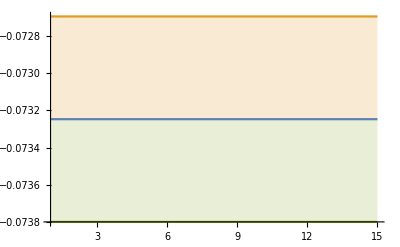

```mathematica
Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,15},Filling->{3->{1},2->{1}}]
```

```mathematica
SpoilHWFLOPlotN3=Show[Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,Length[meanErr2[[5]]]},Filling->{3->{1},2->{1}},PlotRange->{-.1,0}],ListPlot[{Table[{τSteps[[1,i]],meanErr2[[1,i]]},{i,1,Length[meanErr2[[1]]]}],Table[{τSteps[[2,i]],meanErr2[[2,i]]},{i,1,Length[meanErr2[[2]]]}],Table[{τSteps[[3,i]],meanErr2[[3,i]]},{i,1,Length[meanErr2[[3]]]}],Table[{τSteps[[4,i]],meanErr2[[4,i]]},{i,1,Length[meanErr2[[4]]]}],Table[{τSteps[[5,i]],meanErr2[[5,i]]},{i,1,Length[meanErr2[[5]]]}]},PlotRange->{-.1,-0.005},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]],markerlist[[4]],markerlist[[5]]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]},PlotStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau_{\\text{steps}}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3(\\text{mNLO})",Magnification->1.2]]
```

-Graphics-

#### QCD NNLO - gauss

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={393,393,393,393,393};
NWalkers=200;
Nf4α1LoopBig={0.225626,0.225626,0.225626,0.225626,0.225626};
aList={1,2,3,4,5};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
csvData=Table[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"],{xx,1,Length[aList]}]
```

({mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.11737926249916168, -0.11773879446630531, -0.11870203548843952, -0.11913065479036036, -0.11721255244553014, -0.11660297277409887, -0.11730342671581542, -0.11658268055698458, -0.1161226114463324, -0.11687007454597692, -0.11693347849798458, -0.11678312446287656, -0.11738842114256107, -0.11765800331223246, -0.11726689562105821, -0.11815120618669556, -0.11764478406723095, -0.11795152674110534, -0.12058203647114922, -0.11946805826356521, -0.11925885080702511, -0.12130101464330947, -0.12099083428778172, -0.12082655050422213, -0.12105113617704401, -0.12081887456308642, -0.11940140884782707, -0.12132581454549622, -0.1218362878647937, -0.12211819411488246, -0.12363679470983714, -0.12612209291708162, -0.12338960396981896, -0.12163912843472025, -0.12336314986407598, -0.12540901915731426, -0.12356960430936662, -0.1238570322527655, -0.12477038936310447, -0.1251852625807802, -0.12442569411675898, -0.1226420701751785, -0.12270171418609302, -0.12260858447804791, -0.12260965709434042, -0.12178203654078706, -0.12128051741171512, -0.12351854944282918, -0.12215677958029328, -0.12361840632466194, -0.12210595226024243, -0.12252098365502331, -0.12045686663567293, -0.11980026303604996, -0.11905448623778253, -0.11984990645841483, -0.11983654919762415, -0.11962948503059205, -0.11968521171179418, -0.11887158719737889, -0.1199067736845063, -0.1204619286234539, -0.12074870313892713, -0.1205692220061205, -0.12047611972958731, -0.12035986773122305, -0.12126307128552498, -0.12054492364275188, -0.11975091111885305, -0.12067150553035819, -0.12092698282698239, -0.12177869458821054, -0.12285309639132697, -0.12347868411783383, -0.12451732468179746, -0.12308542570079319, -0.12295913271635622, -0.12292150660927649, -0.12194813638719713, -0.12093626561464589, -0.12099847879284306, -0.12123788550269342, -0.12080941413202717, -0.12301673252183613, -0.12163151372779968, -0.12128946712805133, -0.12391995558637328, -0.12551318830632868, -0.12464587709440332, -0.12754324045911047, -0.13111150131104746, -0.1286217395233126, -0.1262824646961002, -0.12373764487759938, -0.12316787691847923, -0.12381562927476189, -0.12308801053450734, -0.12359058888363574, -0.12241576967072924, -0.12285749078209296, -0.12499807585460676, -0.12494129165476613, -0.1260735397714201, -0.12644049165505375, -0.1259671623745468, -0.12433122596132717, -0.1264820249330654, -0.1278154420133893, -0.12564108391478623, -0.12452059510942444, -0.12527046189627247, -0.12801943097385082, -0.12757679874407396, -0.12967528185464047, -0.12831601905110485, -0.12797306170104686, -0.1285493747421337, -0.12845694105460312, -0.12905446942557502, -0.13359800789163281, -0.1287634411981841, -0.13028498069192332, -0.13106480912868274, -0.13129172667255623, -0.12933533093774782, -0.13035999910372423, -0.12912470210151197, -0.1290052041991095, -0.127986678103683, -0.12706316655040917, -0.12660475619941097, -0.128014854270415, -0.12739211822208987, -0.12675276608456684, -0.12466134658703451, -0.12503248987019497, -0.1245883565395611, -0.12371773013506995, -0.12539806988162852, -0.12382990845103677, -0.12620142524515204, -0.12609234812109754, -0.12555870944360203, -0.12388762013702273, -0.12376575300801194, -0.12482905699827358, -0.1261528901529722, -0.13114724447133053, -0.12928401902774106, -0.12874801553840506, -0.1276610841171603, -0.12892706268734005, -0.12915819660238603, -0.12770199792641504, -0.12681809237732333, -0.12862785037281305, -0.12664074069185324, -0.12788270817245412, -0.12967625693034376, -0.1265556488901682, -0.12675920783072514, -0.12849895524488708, -0.1315647712714969, -0.128984264613258, -0.12781413972456349, -0.1278196753672126, -0.12830304814163804, -0.12909553903666748, -0.1332272632074967, -0.13510290809494976, -0.13401084406675456, -0.13070637215276584, -0.13062019254056143, -0.12984053557497388, -0.12698212243170462, -0.12609661870430647, -0.12709342783699998, -0.12555556975923168, -0.12478406289305423, -0.12464953420137222, -0.12634651860184903, -0.12723233791934152, -0.1295959306647997, -0.13071205651370263, -0.1290282958110872, -0.13066758637637657, -0.13152093768520384, -0.1322679880839381, -0.1342288572214541, -0.13768353282263085, -0.1388706516165822, -0.13666243589656862, -0.1386614466558083, -0.1377629830291069, -0.13820628310305544, -0.13389413224014962, -0.13497320545896804, -0.13638356128152757, -0.13590647568968534, -0.13596712756306298, -0.13799147033195142, -0.13670383605592482, -0.14003965465193166, -0.14268048170231395, -0.14230195048201327, -0.14597772646774523, -0.1443702039345917, -0.1455800861645336, -0.14115818921509515, -0.14259994837442685, -0.14898113391891019, -0.14408522696656687, -0.14601913491075322, -0.14493711256174238, -0.15100928895813498, -0.13914254106800017, -0.14663098598229063, -0.14446330838659557, -0.14705893238531317, -0.14393645684223988, -0.14511732477584952, -0.15274108301254774, -0.14974597164279455, -0.17809304139356336, -0.164066095873117, -0.15978421837326476, -0.14479277835631912, -0.1446994296790749, -0.1396749965248142, -0.1437302334446914, -0.15059056503120927, -0.1489272381479898, -0.1450331705062794, -0.14649220336601243, -0.14684833667313502, -0.14717830517656103, -0.14881120853606591, -0.14259272950360766, -0.14418397378894787, -0.14210116367660083, -0.14684838621424542, -0.14433469064003393, -0.14592251229764222, -0.1505604352046856, -0.14844660244321942, -0.16658652349083733, -0.1660884251003862, -0.15029102452073648, -0.14494277198595565, -0.14346329195280882, -0.14633889967739758, -0.14753630796288225, -0.1437967345345793, -0.14442966914911387, -0.1376590210438325, -0.14198066705344203, -0.13454166873375054, -0.1343102598159851, -0.13362486750583266, -0.13111920620280518, -0.13105021016604151, -0.12941434502836216, -0.1275911606512938, -0.12585260145527535, -0.12728352728011955, -0.12776873444188533, -0.1284565925888913, -0.12947452638038986, -0.1355716101443215, -0.13060415959306185, -0.1289231411769311, -0.12685119767513175, -0.12974893210133653, -0.12771381395952558, -0.13149702115501755, -0.13162106556806522, -0.1279268076114521, -0.1259761724634741, -0.1269376853961138, -0.12624842791446483, -0.12639981756325985, -0.12483995842299231, -0.1225895958364692, -0.12406870327127506, -0.12290763261083873, -0.12153946773094618, -0.1198961764202664, -0.12039407453912544, -0.12002688200516969, -0.1187704636810255, -0.11838808629056058, -0.11699446498156983, -0.11874047081128832, -0.11637286550850935, -0.11626063566503483, -0.11895464768255291, -0.11988206286623239, -0.11905785613957424, -0.11817678311128753, -0.11942461914977894, -0.12303446309881594, -0.12348098485350141, -0.12523277968091637, -0.12448088650822543, -0.12108664906233843, -0.1197046714677962, -0.11852964185847902, -0.11932404653080979, -0.11776660966261511, -0.11800640883660109, -0.11739074419092119, -0.11657256134610015, -0.11587812384554645, -0.11562227357962367, -0.11462408229628239, -0.11477668796966425, -0.11398980837518702, -0.11350261040781055, -0.11661105023828633, -0.11496417679863233, -0.11601207317977362, -0.11540830435943775, -0.11462868387888629, -0.11629345814456804, -0.11617193638205868, -0.11615543830699494, -0.11641488594962829, -0.11721829707568765, -0.11956290175976683, -0.1200642914564008, -0.12178774035591236, -0.12110647306178603, -0.11965220063808336, -0.12418606385352671, -0.12471166298360203, -0.12139369392389641, -0.12052647072350914, -0.11968608505434551, -0.11728304368339135, -0.11801680276466078, -0.11634054094727417, -0.11591727012914534, -0.11613778194422637, -0.1168259380847185, -0.1150566856100003, -0.11673113569849407, -0.11861868420773139, -0.12237321176866225, -0.12329468255865926, -0.12232651676251323, -0.11920848085174775, -0.11726967878877174, -0.12032518197122818, -0.11774883988529837],[0.002571464523396108, 0.002375481229765114, 0.002814951659414559, 0.002895357147829324, 0.0025108482484654878, 0.0023479413859409997, 0.00274790755354059, 0.002395539571709836, 0.0023681947780874795, 0.0025660462601978006, 0.0026091480151401356, 0.0025130230024840647, 0.0026081571777992075, 0.0024641095796894847, 0.0023969444107762063, 0.0026295770803444717, 0.0025179452861148846, 0.002547468574153393, 0.0038562140059249838, 0.0032469684983493056, 0.0030607013304639152, 0.003535001587892719, 0.003496872942172883, 0.003145591447160835, 0.0034343030444225343, 0.0031279191694799165, 0.0028461703922352533, 0.0032201090222350663, 0.0033331734816042084, 0.003257769813027716, 0.003384080925957508, 0.00432041553210302, 0.0033514594105892776, 0.003058720935529632, 0.0038413417588156378, 0.004928519700030268, 0.0043968856531818755, 0.004346769629671034, 0.005618155764858485, 0.005274615668248368, 0.004857617169239542, 0.004037023898649824, 0.00370014996512763, 0.0035947477963217795, 0.0037739993937324382, 0.0032991353128614927, 0.0029367251602086426, 0.0039092769351749285, 0.0034568671945061826, 0.0034622635599046675, 0.002959634325275522, 0.0031857164483739763, 0.002665919110492545, 0.002518895964487826, 0.0025950521730445835, 0.002672130814209742, 0.002652244783054286, 0.0025857228282059586, 0.002757518720533889, 0.0023647551198233644, 0.002578440578502202, 0.002699711345243498, 0.002713079651084106, 0.0026342221848392636, 0.002679150599446963, 0.0027055697679341764, 0.002791464301653774, 0.002587256577527686, 0.0025030669716781455, 0.002679802641641926, 0.0028562789283848532, 0.003009163162224186, 0.002966923768212437, 0.003000467323235545, 0.0033261066553072387, 0.003295990208085226, 0.003316220327173888, 0.0036695945457832398, 0.0028645610139129787, 0.0027138670324475334, 0.00262410265343742, 0.0029690908098241285, 0.0030181018254971594, 0.004335535861024539, 0.0035591036737606207, 0.0028214307873469756, 0.003414277093313036, 0.0038097196261779333, 0.003005073050455294, 0.003630764336363025, 0.005903431567472234, 0.00402251059803066, 0.0033119974258497722, 0.002888068556217832, 0.002673695891860725, 0.002788839977223791, 0.002626283464553594, 0.0026365585133546147, 0.002543189340897319, 0.0027559529996770407, 0.0030081086443751012, 0.0029683392320085456, 0.003538633401483666, 0.003769517628794504, 0.003447737971645795, 0.0030571941701825196, 0.003753112734820535, 0.004067892525371181, 0.003211110534072125, 0.003110309363911956, 0.003196240537222983, 0.003927759359386679, 0.003538952045651367, 0.004346410948337483, 0.00399655005387253, 0.004003439414827804, 0.004272853360626971, 0.00409814753934676, 0.0049843632767820716, 0.0086517182362272, 0.004671820268957367, 0.004899977679048326, 0.005224872916023904, 0.005450222848568005, 0.003987436207537665, 0.004088022031245329, 0.004086342428414741, 0.003793672367066905, 0.0036703205286215076, 0.0036129546069209122, 0.003426948218385916, 0.004211661369034218, 0.00410525116931371, 0.004352568733879789, 0.0033942968996060843, 0.0030622165608864306, 0.003299090789139024, 0.002965176975011244, 0.0036071994288099166, 0.002813496721683124, 0.0035553613378207466, 0.0033883382457034444, 0.0033086300575731298, 0.0031276000152168737, 0.002921125355641628, 0.0032656191161018065, 0.003449907577866437, 0.004738473421815378, 0.004244822565957143, 0.0037442928397910104, 0.0033033982109832508, 0.0037686983830584092, 0.003730530364729999, 0.0034484241655019427, 0.0035235288609784935, 0.004344013885913614, 0.0037356502270189393, 0.004108495203527792, 0.00449725421541076, 0.0037408863450849902, 0.004040850668082523, 0.0061174378391827405, 0.007586226775123693, 0.0054955578679511605, 0.005853884837603198, 0.006095601347238893, 0.0066603084421410705, 0.007988452074174557, 0.010742858491229237, 0.011980697966238213, 0.011915178151864266, 0.008721835984948604, 0.0067173162918969095, 0.006288247573610561, 0.004749800804974208, 0.003961766622537939, 0.004853711051370038, 0.003941655044370587, 0.0037077973969164776, 0.003718163465150892, 0.004339007560103271, 0.004395853889112705, 0.005099287812559691, 0.00581429046617758, 0.004862313306977166, 0.005724894813009393, 0.005986467839137507, 0.006999072960633023, 0.0081526954758492, 0.01145091651125849, 0.011997305900485516, 0.010332211011109984, 0.010760723226499102, 0.00966046096864338, 0.009225121807994483, 0.006906227704593038, 0.008528003807301279, 0.009124631196001216, 0.010331366381645245, 0.010946496469884822, 0.01346171600290244, 0.012356622631471649, 0.013414132826367577, 0.017101040892805744, 0.01768083222068747, 0.01744888513654023, 0.01904030983743835, 0.018599084701984146, 0.015033419930685799, 0.015553488800589594, 0.021976737727444823, 0.018101861757292434, 0.019823982955978096, 0.01775115230936775, 0.021625187701098697, 0.012373496983365427, 0.018184981098791884, 0.015784967005089138, 0.017342497438861643, 0.015971848637573966, 0.016712990479480466, 0.020217382359415524, 0.01899659239093867, 0.040406679611526164, 0.028838228185707238, 0.02638180713109173, 0.01638361443363065, 0.016629480370966735, 0.012749422759539253, 0.014714715564137058, 0.018425765077173157, 0.01640660696977128, 0.012723859654344997, 0.014384403233516802, 0.015568150961460669, 0.014348231128142848, 0.015471277365090772, 0.011645102706124304, 0.010515881376746528, 0.008725863571164446, 0.011846691651551616, 0.010156762733599702, 0.012681712358128776, 0.016240226715769367, 0.013929364938926133, 0.02506137557132404, 0.024961554532613874, 0.015393941802823762, 0.012221102896516563, 0.012705815686418126, 0.014083304891215297, 0.01590324221258855, 0.013232735420796029, 0.013453900000965097, 0.009497078169639414, 0.011232288883991366, 0.006729237222663347, 0.006087966713781817, 0.006263599112431452, 0.005248885840119085, 0.0057599206161918146, 0.005397362387351323, 0.004529449885485917, 0.004275399429070597, 0.004780085802058786, 0.004346069227603182, 0.004107124045053923, 0.0045548052855824235, 0.006979012123442542, 0.004408634436182933, 0.004033433971643417, 0.0034033578153821135, 0.005126372554668012, 0.004154747296912526, 0.006293362246735051, 0.00631650280397383, 0.003841309512158143, 0.003170083609015306, 0.003360363721297352, 0.0031103420528868445, 0.003058179983251581, 0.003794113917762873, 0.003016117317304482, 0.0035471426837623108, 0.0032434425412895076, 0.0034995837738450233, 0.0024945144845766563, 0.0035329090960476684, 0.004203737370888417, 0.0036716294735067113, 0.004075669810055592, 0.00447405564437364, 0.004401538435863723, 0.0037380118650251594, 0.0043257697099578375, 0.003905951694048833, 0.0029841664436045445, 0.002248428577298759, 0.0028355406973662118, 0.0025671065342172486, 0.0041206102683487705, 0.0035870994170299204, 0.0038937634370912974, 0.0039039122148960565, 0.0028937526542924205, 0.0029676747673124952, 0.002636377037681071, 0.002470551419235149, 0.0024442115799686733, 0.002522402126711291, 0.0026473448719256014, 0.00308329094964688, 0.0031083383102835315, 0.002594852455642363, 0.0030884201379969512, 0.002860445976683303, 0.0035150478805989127, 0.0032385416444216525, 0.00241311913737997, 0.002242063988055274, 0.0023311503023820696, 0.0022470638607147084, 0.0022514282211353017, 0.002429093936374248, 0.0026307057141537627, 0.0029735254266295952, 0.002933492838265309, 0.0032343100088077776, 0.0035402530421207563, 0.003749826343254314, 0.004623688922850165, 0.004349442427131483, 0.003976642932764244, 0.006050285629895608, 0.006280034080752536, 0.004457805439415505, 0.0039025268588176263, 0.0035445303063590117, 0.003902832364950715, 0.003871662543676599, 0.0034757309111246165, 0.0031043222687230443, 0.0038536000656001035, 0.0040802089478823925, 0.0033805613500852557, 0.0034183682718800057, 0.003198255741182631, 0.004175939797131248, 0.005265515143727998, 0.0045134659019357955, 0.003827625663094251, 0.003035465905167211, 0.004717144942253317, 0.0036308532639822296],-0.118336,0.000650625,0.405698}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.08190699762173155, -0.0817860899851993, -0.08196662877893603, -0.08300233273109049, -0.08289581082995158, -0.08263227906936067, -0.08310829388631014, -0.08393601110477121, -0.0852510734735789, -0.08617321651530326, -0.08555204672312439, -0.08537205769038725, -0.08727092628539233, -0.08570431877801868, -0.08480620714124217, -0.08387153994865214, -0.08439790922502649, -0.08417764989121888, -0.0839383006904982, -0.08374281622620554, -0.08421354420806461, -0.08416958127402605, -0.08426383534903706, -0.08479442693048889, -0.08523203038127718, -0.08644485209686106, -0.08689159452602022, -0.0865608163023857, -0.08576859833933219, -0.08579283525293074, -0.086165586838753, -0.08582707178925343, -0.08612862224062277, -0.08654132071223004, -0.08703616054524727, -0.08762518816547948, -0.08834153563219846, -0.08832972152095904, -0.08861617768651872, -0.08784973786513398, -0.08779007406930237, -0.08761716608196783, -0.08721753716915429, -0.08735169782652613, -0.08746809081686593, -0.08770210164834369, -0.08817170606787164, -0.08903987008315406, -0.08923158685209662, -0.0901085114950745, -0.09003809078766024, -0.09072674933221898, -0.09072951193899206, -0.09033472393676369, -0.0903813373322559, -0.08976354774477602, -0.09057378501728437, -0.08957526836051712, -0.08966483273173498, -0.09026009151928918, -0.09024417694573086, -0.09050391132573456, -0.09164086847066209, -0.09049892092254264, -0.08958644924901234, -0.08935324857308082, -0.0890359857069716, -0.08831152813340112, -0.08808694643203449, -0.0879851342100354, -0.0882307853224777, -0.08850108683046792, -0.0888958911657814, -0.08959676953616101, -0.08978669141792421, -0.08952873836741801, -0.09014350491894907, -0.08945484032646142, -0.08911393720644872, -0.08939073130681312, -0.08968025297440212, -0.08995938803342458, -0.09049022195221418, -0.09135063852678096, -0.09180126607169208, -0.09182687001441092, -0.09227063867070835, -0.09208036195558872, -0.09292489281620923, -0.09398043158754112, -0.0938083688388584, -0.09384861258302357, -0.09406255379644984, -0.0949897975237997, -0.09749952975167231, -0.10310989692709209, -0.10003836112327777, -0.09825831096220755, -0.09901949379434721, -0.09725824082713863, -0.09736542286114411, -0.09671789884175494, -0.09570641336882231, -0.09599426633214272, -0.09539418674481953, -0.09452943310779416, -0.09485017840904429, -0.09469418259148224, -0.09425887556828137, -0.09399432524933753, -0.09451982546255686, -0.09423989940671146, -0.09447202269973255, -0.09510021159467617, -0.09446842105534488, -0.09411072488251741, -0.09470498109488637, -0.09497046572897552, -0.09468744303579774, -0.09505093681860007, -0.09503459638292037, -0.09611826740235686, -0.09561819543154924, -0.09528503960640966, -0.09541894971676358, -0.09667800982915244, -0.09935940691193414, -0.10174916569405515, -0.10186195025870483, -0.10105418845979251, -0.10015551409405296, -0.10167622198461258, -0.10027199577471949, -0.10100190737848201, -0.10110885111119784, -0.10151191650369007, -0.10024693165401136, -0.10000193049209785, -0.10096741417439097, -0.10376922587880086, -0.10285869635798739, -0.10173810657832429, -0.10448364701597254, -0.10317472335260999, -0.10103941322957115, -0.1020211608600228, -0.10396455983425633, -0.10447030011068555, -0.10650579438679278, -0.1076848588058549, -0.10776635119739814, -0.106306109140681, -0.11152642920630931, -0.11224499387183817, -0.11170410816210209, -0.1081039688139176, -0.10621444586139786, -0.10585034548316645, -0.10726091885542774, -0.10708602492370294, -0.10624505938433335, -0.10457574448180432, -0.10618245980041165, -0.10552880801470046, -0.10366617917915898, -0.10600790028450342, -0.10756146803750047, -0.10885421818073128, -0.11059873826735471, -0.10720521036960833, -0.104151041747984, -0.1043726342648821, -0.10449682229038842, -0.10390243809964116, -0.10479305154370742, -0.10556944672158299, -0.11229003453264733, -0.1140682086462963, -0.1141878514717997, -0.11435523083064701, -0.1150285528148022, -0.1264509106857391, -0.11749477873280444, -0.11158372173095006, -0.11694757365264731, -0.11796756524245582, -0.1149305160059152, -0.11760730362900984, -0.11536828077441917, -0.11284823881850775, -0.1121898298771645, -0.11449376421754677, -0.11461500357351208, -0.11327603780128385, -0.11641566030889898, -0.11345999411573326, -0.11494537725019362, -0.11330152446090368, -0.11272534118670037, -0.11187595022603965, -0.11008477057906034, -0.11176475993803273, -0.1120588532356979, -0.10929753621827665, -0.10915217531252272, -0.11032132768662657, -0.10967436930340066, -0.10986028969992181, -0.11056009567327646, -0.11270808998011858, -0.11189571936337342, -0.11297809710683723, -0.11141346967715682, -0.11234132106741694, -0.11497891932384932, -0.11215906579253407, -0.11113631823209931, -0.1100225545164435, -0.10812106187065793, -0.10860683541330901, -0.10942984050843768, -0.1096831956439573, -0.11132425725126167, -0.11198862409576991, -0.11299250695095683, -0.11471189111644796, -0.11203078175388637, -0.11338726124492284, -0.11425481359469036, -0.11469215682145112, -0.1143032667148455, -0.11423724550175694, -0.11824154909955524, -0.12445415871349534, -0.1291372760224178, -0.11897867097132785, -0.1193114319825678, -0.11916065448090656, -0.1169472792959414, -0.11709591179407806, -0.11883215405085694, -0.11737723598740503, -0.11441243960328777, -0.1131920952559747, -0.11238290579432333, -0.11303524578199456, -0.11317335884669608, -0.11246655607450817, -0.11128185301988072, -0.11055593468449297, -0.1094954479264322, -0.10912382432568257, -0.11061813097293276, -0.11021274134927582, -0.10851290260182019, -0.11020948142646517, -0.11182108794311282, -0.11202314521027229, -0.1122687580532119, -0.1122058623446089, -0.10983984686049642, -0.10848480278342193, -0.10863399840305595, -0.10924964375294036, -0.10776389882041246, -0.10680708141325707, -0.10712149781768844, -0.10736909786160966, -0.10697790867136114, -0.10554943087826554, -0.10450616485941408, -0.1045271045303652, -0.10648712038916597, -0.10736195344588494, -0.10767061391705685, -0.10819581376923303, -0.10830978035039014, -0.11018657889306985, -0.11182882454341202, -0.11190463197805868, -0.11073259051148707, -0.10944983624933255, -0.109058729983566, -0.1096207017114125, -0.10888701545128118, -0.10704929935251693, -0.10549741846539559, -0.10589535350949414, -0.10579795590514705, -0.10527969836796666, -0.10360981836574445, -0.10478287982976023, -0.10610902499286143, -0.10446827396539207, -0.1047219940674284, -0.10645847457541913, -0.10674025032603705, -0.10640146648300641, -0.11040813710016774, -0.10806876601351291, -0.11011417928634427, -0.11061062226467815, -0.11235964833732708, -0.11615062395298718, -0.11488223241906408, -0.11669652145406065, -0.11671523949163687, -0.11756041943002363, -0.11895966798372747, -0.12127965344919056, -0.1296051834892659, -0.12015055375768036, -0.12004106440708802, -0.11624285148846861, -0.11711324641692593, -0.12179236964186918, -0.12751024418920662, -0.12169328840492699, -0.11816837273776944, -0.1188710706240564, -0.12138130442678677, -0.12425790885038882, -0.14003824577234456, -0.14623795174728585, -0.13939857313933174, -0.14454645851048545, -0.1367519297905259, -0.13111519514445866, -0.1211393532945727, -0.11839884963778409, -0.11549572833737763, -0.11309639792008282, -0.11082895096666101, -0.10971706610215658, -0.10924373388678657, -0.1088573487175575, -0.1112595898921651, -0.11003092098518905, -0.11161179197101131, -0.1122933770202033, -0.11247119346524125, -0.11184422851677601, -0.10888431828001122, -0.11076683509957345, -0.11113741941562591, -0.11229767444897061, -0.11266754564201951, -0.11414138171903937, -0.11305887135807807, -0.11610472565614662, -0.1127785652711651, -0.11247103384912199, -0.11554373302893318, -0.1147214702469063],[0.0027870238591020478, 0.0025897614195263346, 0.002745695814258691, 0.0033651237461273, 0.003034217581107082, 0.0026835659415363265, 0.0029787953232005993, 0.0031631326510830828, 0.0038342834360157695, 0.005278638019016329, 0.004469040837431254, 0.003905732957157717, 0.004746396322271855, 0.004301284242795049, 0.003956741126769554, 0.0033156434321734503, 0.004011419844438402, 0.003545732948995735, 0.003217805475782684, 0.0030938651127140077, 0.0031362462039389097, 0.0032998878484505867, 0.0033469464538813196, 0.003709896345021691, 0.0038496064713267704, 0.004670715214583301, 0.004957023901288197, 0.00448715371405434, 0.004127516977057598, 0.003908009612016828, 0.0038393900925253717, 0.003685527720674465, 0.00357882152970575, 0.0036785987651257036, 0.004179214167847662, 0.0045278607438607186, 0.005017453719356647, 0.004914755697620501, 0.004796105894695541, 0.004237001414970148, 0.004293915081856855, 0.003931942229012539, 0.0033789074415436606, 0.0034698776306059066, 0.0034001598436930094, 0.0033453273290934083, 0.0037506853206999025, 0.004147437882212567, 0.004298301909359995, 0.004607895202321145, 0.004403373101337999, 0.005062617280349917, 0.004990034415536185, 0.004622036941480433, 0.004523947238501991, 0.0039336500656762564, 0.004455710685742095, 0.0038558159234481433, 0.003996008904832077, 0.004409795756958853, 0.004300722900377638, 0.004441252976788802, 0.004977386706483577, 0.004569954996846235, 0.004059715453499728, 0.003959009644599097, 0.003696514274162849, 0.003321083461174689, 0.003246911004159624, 0.003151302712526197, 0.0031155103231194597, 0.0031707831791075607, 0.00314676981108373, 0.0034320071855026032, 0.0034413797043598058, 0.0035085817744926733, 0.0040971331126713, 0.0038204260004870596, 0.003970908721088022, 0.004106981790297208, 0.0043007335067315605, 0.004474201749610559, 0.004577552639516381, 0.004948501767062211, 0.0050659580428109, 0.005067100800026818, 0.005111240342581249, 0.0050166281724278936, 0.005448552875527072, 0.005843331473536796, 0.005212273197423928, 0.005149993231788433, 0.004861545572125692, 0.004976007930033443, 0.006007617523692546, 0.009150399771023113, 0.007424081135963333, 0.0064134597080410935, 0.006432725150189454, 0.00575131032071303, 0.006012765080552886, 0.005761445571552594, 0.005338331285836587, 0.0052541484651149155, 0.004904124482908565, 0.00455087980182983, 0.00451305356234897, 0.004574985679116253, 0.004339980660471812, 0.004283773588660751, 0.004284879041141714, 0.00418736477518903, 0.004397320819796166, 0.004506829645779368, 0.004200389274220687, 0.0038544582600916876, 0.0037845910374939757, 0.0038675000108187325, 0.003627915458987343, 0.0038287261907726444, 0.0038409480405793756, 0.004271791698356612, 0.003981969144442837, 0.003972536887398951, 0.004155434659840226, 0.0044823927386230455, 0.005815972008938288, 0.007116968061330693, 0.00694723189704655, 0.006617509273952332, 0.006208301525321534, 0.006951322354557285, 0.006083366953712092, 0.00672059050184021, 0.006359070578193849, 0.007085372095126803, 0.006229888291677459, 0.006055236157853409, 0.006364159215736115, 0.008321400905824774, 0.007971039168028424, 0.007466736912185294, 0.009019297706488913, 0.00804116406250182, 0.006746146175854287, 0.007108567412431231, 0.008067453941679946, 0.00795929456666747, 0.008852485629613521, 0.010204979000165329, 0.010326693599415454, 0.00976823296361926, 0.013592820409430316, 0.014705616508757652, 0.014094071337760269, 0.011312027361074416, 0.009309695848441126, 0.008984744372335342, 0.009155617726755806, 0.009310728568088967, 0.00832661933247691, 0.006748177125080104, 0.007170841663423414, 0.006549405656684086, 0.006045459828097502, 0.007305416803609753, 0.008442981010376827, 0.009203372863887421, 0.009880178328803647, 0.008182794476592967, 0.007314494666133909, 0.007273319714128766, 0.006662832030738141, 0.006275398179467061, 0.005906882580128318, 0.006314020960066045, 0.010080610312222014, 0.011056836129488263, 0.011694824547108244, 0.011963706332642623, 0.012109606765621573, 0.020109945746255267, 0.01384170875363678, 0.009699636533423558, 0.01268199761217183, 0.012286173262120609, 0.010224033932769865, 0.010434089768498946, 0.009092700919136857, 0.007741707091386298, 0.007480374803054348, 0.007781184403880291, 0.007952548031146403, 0.007915915900186192, 0.009436873263771978, 0.007760896779042729, 0.008391656488412178, 0.007737731454931811, 0.007403482947775603, 0.007394065442018783, 0.006402509845696709, 0.0072829974731852725, 0.00768809028740175, 0.006553515871152078, 0.006630198842331123, 0.007059900010743821, 0.006452701022215356, 0.00642459661634546, 0.006511107436695673, 0.007388093906531115, 0.007415852337549893, 0.008157947754760137, 0.006976599997122875, 0.0073829395816147605, 0.008148028307336214, 0.006604289359585085, 0.005985224560967592, 0.0056564186888198, 0.004768497139780413, 0.005126348486490345, 0.005248084385586694, 0.0052605227644209225, 0.005311886342426104, 0.0055492350933378735, 0.00569015071127562, 0.00630183765866397, 0.005579632662030742, 0.006154157112428467, 0.006434154216093849, 0.006546741885763222, 0.006929785368824352, 0.007317248281774104, 0.008871848856863353, 0.013661671985328371, 0.015892143217358014, 0.007489355685342307, 0.008080242216037476, 0.008286732581801726, 0.007701817381912102, 0.007882516196817395, 0.008824501194869222, 0.008565563535096792, 0.007019451316186082, 0.006713839035086384, 0.006729341836989338, 0.006465073479449542, 0.006741193459788785, 0.0063347984792351585, 0.00604616687344248, 0.0056852456635077125, 0.005275041755041551, 0.005333995746977862, 0.006517738796012157, 0.006483137809710544, 0.005365231784757819, 0.005654915386295761, 0.006709497260836312, 0.006557991981403504, 0.006807054880392289, 0.006776868779020072, 0.00716629942937461, 0.006527606206445774, 0.006766088353333171, 0.007266623318980323, 0.006784077602220618, 0.006465551527951262, 0.006154020425003913, 0.0069944808210960765, 0.007127108615186718, 0.00642234927532264, 0.0060620930930994936, 0.006451396136940298, 0.007095853764625993, 0.007869883654443318, 0.007977073140994809, 0.008442405014223352, 0.008047050280054709, 0.008517008399712405, 0.008586696371754788, 0.007999081672443873, 0.008643991568083919, 0.007510285439584333, 0.007387325241726845, 0.007733146306180756, 0.007516909537564441, 0.007870096345435822, 0.00795673146925254, 0.008346285666487261, 0.00826110986990938, 0.007634621859237795, 0.0067326060321461325, 0.0074036107922493145, 0.007935395450446104, 0.007579808056085717, 0.00794823646186268, 0.008551721515457142, 0.008732739026646482, 0.008369664674612849, 0.009832515899448715, 0.008750711383013582, 0.009650699240679957, 0.009707300881783164, 0.011419774055360913, 0.012546544174183164, 0.01193291896719463, 0.01302167276412342, 0.013279765932822788, 0.0141971630596985, 0.01436350674099912, 0.015806666906185846, 0.0230594516711945, 0.014731072978552648, 0.014499595884870197, 0.012497119362591668, 0.012426151488526953, 0.014439077400501791, 0.018694946898196802, 0.014939552903449158, 0.013320748235173202, 0.014883823804919826, 0.017579898740562108, 0.019126771203566078, 0.028678459452486454, 0.032344169055412327, 0.02674524563401768, 0.03181348703700103, 0.02371958316956755, 0.021182295254690918, 0.015383852113156425, 0.013451630813815936, 0.01196738226290674, 0.011272482912875036, 0.010615365050204138, 0.009713212902469777, 0.008682348526586184, 0.007995805160826647, 0.008514060473276311, 0.008181712101283933, 0.008962711338337618, 0.00872735412186353, 0.009230364975230032, 0.008913378109605, 0.007158285093577342, 0.007839600712186935, 0.008189530982543977, 0.008277814816664696, 0.008441590482183622, 0.00870986558478166, 0.008537397349577938, 0.010699316684444274, 0.010777583986149575, 0.011003457515717293, 0.011062340357636568, 0.011629471321004864],-0.0829323,0.00120908,0.306723}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.06194000151336742, -0.06188169275533064, -0.061918450688063724, -0.06211768428597966, -0.06208840925019255, -0.061949617068236984, -0.06196003164446379, -0.062350702208542816, -0.062349805304214606, -0.06254093297444101, -0.06250283505754112, -0.06270456732351765, -0.06289507196017598, -0.06273226481755476, -0.06258110106751286, -0.06266435351842245, -0.062406348323548154, -0.06242030431363355, -0.062499889973753865, -0.06288367313102593, -0.06290268589703932, -0.0628757268735553, -0.06306611691094029, -0.06305196213208779, -0.06305279259810541, -0.06318113394698349, -0.06338598262644002, -0.0635347051644759, -0.06352042332424476, -0.06353034911410464, -0.063513066072701, -0.06349922150663972, -0.06364417482800289, -0.06344803414006327, -0.06341093059542717, -0.0636027785562052, -0.06377345392608878, -0.06393101715951958, -0.06390507485041866, -0.06405840042722896, -0.06403778688653596, -0.064069312734906, -0.06410726177463778, -0.06425707960506517, -0.06429312336484361, -0.06448712810879093, -0.06441792649625817, -0.0644341468474153, -0.06453758822992955, -0.06486811243128957, -0.06507818076192926, -0.06492648346279191, -0.06497266096491239, -0.06504368481308755, -0.06502062869900405, -0.0650614875750694, -0.06503180582453075, -0.06517580567224557, -0.06502659773202096, -0.06518042447091922, -0.06506562646358255, -0.0652267005751728, -0.06530732851229543, -0.06522517681351289, -0.06531807247726396, -0.06553064724185571, -0.06568593704247838, -0.06565882183481807, -0.06595185038379082, -0.06591551315852781, -0.06585019500842355, -0.06586554648349657, -0.06632965653700426, -0.06637706109797634, -0.066441531739126, -0.06683762006804253, -0.06715937953473082, -0.0670863894396601, -0.06766180398303114, -0.06850982447717069, -0.06898064523521759, -0.07123115102696312, -0.07205170466212638, -0.07184913511038714, -0.0697636176535848, -0.06900405730784444, -0.06870228487168811, -0.06847174535694928, -0.06892844403485111, -0.0693133812064746, -0.06966866567191225, -0.07018655088649767, -0.07043213828278296, -0.07011895971278562, -0.07008378462954844, -0.07110023245012478, -0.07072883607778166, -0.07103704811418415, -0.07098378610168607, -0.07075255237463547, -0.07106118065405366, -0.07098729917738948, -0.07065458894203222, -0.0707807709449962, -0.07071517790284239, -0.07067129285748457, -0.07087596848794174, -0.07069605237566617, -0.07054815797763593, -0.07031456491402636, -0.07046338733960904, -0.07084597822368992, -0.07086206626192436, -0.07108573408826396, -0.07080232136016458, -0.07124838738961713, -0.07198840684117057, -0.07194464458158666, -0.07193601015098915, -0.07299390223490353, -0.07328617987503949, -0.07346379306791133, -0.07311866697111032, -0.0729075521167082, -0.07308955970228197, -0.0733629430404076, -0.07369089507623042, -0.07442264469630791, -0.0751654304293465, -0.07534545381807252, -0.07608030411990195, -0.07554421613092673, -0.07709926400515067, -0.07580070352346709, -0.07449594556936574, -0.07500890454316218, -0.07561579845124643, -0.07587076518200632, -0.07586950495656715, -0.0760910616708805, -0.07638973075216, -0.07547438068936164, -0.07546763056956025, -0.07699488367172348, -0.07749167449385606, -0.07649380387262897, -0.07607445775685358, -0.0765770453593582, -0.0763916063087308, -0.07706000462598797, -0.07664936049750927, -0.07701624222541398, -0.07656569179983579, -0.07644789928144238, -0.07732621247891425, -0.07891462386834955, -0.07927136394761476, -0.07963316002917599, -0.08017224757028706, -0.07961071403892592, -0.08461225640372545, -0.08466644572251236, -0.0849378080624091, -0.10159929413684526, -0.08457087130316628, -0.08192476237977797, -0.08242154998523292, -0.08382457184542291, -0.08404537026092258, -0.09021447503047703, -0.08682295209400034, -0.08591478530776975, -0.08582329417831001, -0.08557633003311871, -0.08930305993539202, -0.08774267707711828, -0.09025094571777209, -0.08736478670900855, -0.08839656611213494, -0.09474406166738697, -0.10404657367221018, -0.09831261209319325, -0.09766167403729974, -0.09266002095168013, -0.09211457347194334, -0.08966190748153048, -0.08915604732478197, -0.08871260013042033, -0.08577445770957834, -0.08742645079690034, -0.08619865239717392, -0.08832789288291798, -0.08811728360574264, -0.09488758658373829, -0.09190225430827274, -0.09031717347409458, -0.09186803363667126, -0.09557412097306558, -0.09961771933184561, -0.09480902318241141, -0.09402649328385361, -0.08940960110691343, -0.08947839501414323, -0.09438921960071413, -0.09512182413927626, -0.1030703703567754, -0.10548863750980485, -0.10485522766677291, -0.1221884832219248, -0.11061226769267071, -0.10315923030655753, -0.09941472017034086, -0.09293055697173606, -0.09287308003632462, -0.09405033648999693, -0.09366323074683416, -0.09440238954384596, -0.0905320263807736, -0.08924903482761531, -0.08905910283064297, -0.08877776064640522, -0.0867490198176337, -0.0870264173943205, -0.0882692980398172, -0.08598149052430841, -0.08559452944385272, -0.08499281389363218, -0.08429557190919966, -0.08394715707838311, -0.08361545193826685, -0.08359304329203696, -0.08294242809483122, -0.08306901744273722, -0.08278197798666899, -0.08281204402796827, -0.0833279378070203, -0.08307948384461847, -0.08319677537997332, -0.08288651290859823, -0.08297945900922085, -0.0830927875271919, -0.08476110035233159, -0.08502788245533456, -0.08420562446841287, -0.0834640597229946, -0.08329471240593429, -0.08450122167132049, -0.08382584734019356, -0.08365817236159431, -0.08299627706397884, -0.08291141168794104, -0.08356197996623027, -0.08361519475328505, -0.08407094189193512, -0.08528715808234512, -0.08468265237644895, -0.08554065388159128, -0.08615652028894731, -0.08525597646014828, -0.0841242685445513, -0.08433819686310182, -0.08383889071653762, -0.08454848823371644, -0.08595065591904784, -0.08590246518452975, -0.0848409343679271, -0.08510603801881275, -0.08536319890053326, -0.08614390957450165, -0.08631996934101768, -0.08626408970342699, -0.08646688913724133, -0.0879927149023462, -0.0874006212245979, -0.08846161128043455, -0.0875450380499958, -0.08693007538566055, -0.08631068246125231, -0.08722794851248614, -0.0887908030869724, -0.0895095275258625, -0.09061794144355435, -0.08956012139549116, -0.09119384955890449, -0.08872278622405487, -0.08673978488759453, -0.08430915039815598, -0.08420763007271422, -0.08467896347110505, -0.08490439630674584, -0.08499436100596192, -0.08595756887547759, -0.08578020521651561, -0.08538532677965142, -0.0848200194391698, -0.08428158476557605, -0.08538427923314602, -0.08520253520463275, -0.08455823677913897, -0.0845867238236512, -0.0845861289225896, -0.0842715532103949, -0.08477208129250047, -0.08447968043172074, -0.08345776128971163, -0.08387756720221144, -0.08467566836648673, -0.08492190703468727, -0.08584217148372704, -0.08609820419352215, -0.08580841835825435, -0.08483670702310508, -0.08455281653325672, -0.08405433015906717, -0.08494506453664143, -0.08503080728138736, -0.08604864059993009, -0.08630586299807927, -0.08590525022832408, -0.08669020585480931, -0.0865747817069824, -0.08609100505947148, -0.08662905233944194, -0.08666167924699358, -0.08702389071962563, -0.08799973291448322, -0.08718774281693417, -0.08728273372353998, -0.08852722550806891, -0.08820020079298337, -0.08805340816991807, -0.0889534340462414, -0.08893509223648285, -0.08881998254842609, -0.0896378597770064, -0.08988383603019516, -0.09133701503904776, -0.09174211474984781, -0.09065668791425659, -0.09005288098668555, -0.08955547868512698, -0.08979952720301225, -0.08847596992610747, -0.08839300745679418, -0.08731545301948763, -0.08680774839076605, -0.08660627097897038, -0.08650750058474851, -0.08661833136924003, -0.08535014741748083, -0.08544687711545049, -0.0844903471783323, -0.08506328355369874, -0.08572025720963415],[0.0015107847679422454, 0.0014272377358562625, 0.0014264972699175131, 0.0014717665059554976, 0.0014731684970252178, 0.0014297366802122542, 0.001424677246414113, 0.001501716941845502, 0.001475465008344743, 0.00163631127486956, 0.001574558758785076, 0.0016042645627614876, 0.0016049495476753515, 0.0015166854889036396, 0.0014844269984533465, 0.0015272848136667764, 0.0014288184147838174, 0.001411934196258017, 0.001428519492398136, 0.0014946317575544304, 0.0014545007427265682, 0.0014318713357220165, 0.0014783615623170186, 0.001470090456787711, 0.001460361828179232, 0.0014573691803523785, 0.001476870498666753, 0.0015240205299821476, 0.0015492363178397281, 0.001516991898243113, 0.0014603406555004255, 0.0014626553594864942, 0.0014754874908066563, 0.0014305681066905658, 0.001390593771458828, 0.0014292867621662165, 0.0014308471731853541, 0.001455766787218206, 0.00146992646550313, 0.0014816307107391713, 0.0014688923068258797, 0.0014590100895985995, 0.0014677692346067252, 0.0015186573307754618, 0.0015682394235940937, 0.00156864424162054, 0.0015714743393679053, 0.0016122460646140304, 0.0015939040490826136, 0.001650949339292892, 0.0017032960474504184, 0.001665978676913145, 0.0016960341610542991, 0.001681293091710485, 0.0016507602386029321, 0.00163756637961009, 0.001642573831964225, 0.00162413398778074, 0.0016056989463727848, 0.0016864963235490406, 0.0017014521493954498, 0.0017574499601389713, 0.0017928149793725822, 0.001824607290337016, 0.0018739258329979643, 0.0019465705425220717, 0.0019505204480395626, 0.0018755566566017797, 0.0020320145197861485, 0.0019528899184533212, 0.0019405952525883036, 0.001906216367870011, 0.0020144554637931155, 0.00195889895300641, 0.0019368928911117935, 0.0021101941965505707, 0.0022662781831893266, 0.002248725567740357, 0.0024280185384742826, 0.002854534591881622, 0.003174711781421082, 0.004710186793401646, 0.005717278891744599, 0.005414684527216202, 0.003730486343696379, 0.0031049228436780658, 0.0029318845130185717, 0.0028213715526547037, 0.0030005846388298104, 0.0030221639429871315, 0.0030502822814891797, 0.0033363313640210786, 0.0034780746087477244, 0.003255505011454567, 0.0030639760278362983, 0.0034594194409921686, 0.003296013581667679, 0.0032907233205361174, 0.0031345588697471623, 0.0030814178617612487, 0.0032224447891107404, 0.0031454255354330584, 0.0031188623540778578, 0.0031282136528269673, 0.0031491783221906126, 0.003125563583087255, 0.0030781076104173066, 0.0029985732397658925, 0.0030750364050883706, 0.0029737729924922407, 0.002921885285042597, 0.0031030599196955116, 0.003109522835470261, 0.0030789389567344922, 0.0029622047213882516, 0.0031455407116635758, 0.0034033285273217233, 0.0032269451964469266, 0.0032473656739195186, 0.003611387646402405, 0.003697321577944151, 0.0038166817626891767, 0.0036132811493157922, 0.003378746721075454, 0.003405312078821594, 0.0035823898560008137, 0.0037568041521615445, 0.003984857683592253, 0.004313263245823007, 0.0042523319794963346, 0.004633774586509191, 0.0044793587562999785, 0.004923816391542231, 0.0044436260546651864, 0.004082939408676852, 0.004270950654201109, 0.0044694555405444215, 0.004773106808737205, 0.004650130908085695, 0.004759630202951197, 0.004866967056524397, 0.004436062199000052, 0.004310555077831675, 0.005035871925814306, 0.0052322709522164956, 0.004729979261166156, 0.004549973980508579, 0.004847749553154369, 0.004947876636609414, 0.00539788037081572, 0.0049144692445487045, 0.005159441845291015, 0.004624021214689575, 0.004243093332887088, 0.004687916861831946, 0.005583017195645819, 0.005779953227541848, 0.006035968629547372, 0.006108806463945762, 0.0061258426830923, 0.009186521147594126, 0.008806795984001189, 0.009040244688551536, 0.02405527852343288, 0.00921767179363303, 0.007834776223123265, 0.007690976285577054, 0.008886074555076486, 0.008678799367418891, 0.01423350771711575, 0.011415463700891009, 0.010566407454781681, 0.010382228791262282, 0.01040012198723261, 0.012950644528669595, 0.011606257661172155, 0.013317258270350862, 0.010505149898961886, 0.011240836770833746, 0.016270789314459654, 0.024506593270238197, 0.017397950812068134, 0.01677718024815685, 0.013757232645978138, 0.013395020900370192, 0.01128036331787689, 0.010383122656777365, 0.010251563591059233, 0.0085754648653765, 0.00953359563628929, 0.008572414464159505, 0.009895472086463325, 0.009646943410370049, 0.014817348722494173, 0.012364840170455572, 0.01134495005434157, 0.012190761741067375, 0.014288237624100187, 0.01681326591465328, 0.01303935702938312, 0.01271430481325225, 0.009762499111296084, 0.009992069707919347, 0.01344621519712544, 0.013422328429757283, 0.018773656480568644, 0.020089009874158816, 0.019671093442895044, 0.0337361769353118, 0.023190155481050554, 0.01781225741285224, 0.015163308007239076, 0.01098022642583767, 0.010871836799538919, 0.01134168171859873, 0.011121256972819455, 0.011598112437700701, 0.00901507777917652, 0.008137163186300866, 0.0080790850949077, 0.008208319435558031, 0.0067199078867242225, 0.006846404279913708, 0.007609575257741035, 0.006480096909904195, 0.005914339572189669, 0.005754591972420678, 0.005476161639358535, 0.005472474197929944, 0.005410698836732918, 0.005553196292675293, 0.005162506967544602, 0.0050172418816258595, 0.004705397055430209, 0.004692074835415617, 0.004917804648579111, 0.004549630806925397, 0.004750482998670451, 0.004698455618278493, 0.004812169670501495, 0.004816918496199344, 0.005492177688202101, 0.005897637742025916, 0.005518288559074648, 0.005207766791234711, 0.004944991674133421, 0.005446986385161261, 0.005218374347460543, 0.0051138159808946995, 0.0048565022744753395, 0.004772910381798931, 0.005115038877051498, 0.005014965815871527, 0.005198614781030171, 0.005429379021777126, 0.005165975269232954, 0.0054582319398020765, 0.0057499225582774765, 0.0053662702315646175, 0.0050593246605152, 0.005226616310630347, 0.005206711657459489, 0.0055013247022177554, 0.005864777619466138, 0.005872477552026021, 0.00560780267481681, 0.005505128920163802, 0.0055644389263989884, 0.006053040522261797, 0.006226448689806313, 0.006068079249542114, 0.005979222616329279, 0.006491041952882502, 0.00646597806580672, 0.007177485718050954, 0.006682345723761742, 0.006604086684219044, 0.006369146245539533, 0.006691019495226654, 0.007101955205026723, 0.007367587075876276, 0.008033823689612087, 0.00765480206389037, 0.00835869980992597, 0.006955797377283353, 0.006257221649759465, 0.005536980748764467, 0.00530274125715041, 0.0053934923043564694, 0.005586517315990396, 0.005469541240663945, 0.005817857474155518, 0.0056506948143367815, 0.005686499059407132, 0.005508362793701843, 0.0051410780003310185, 0.005587336354973335, 0.00547882443189441, 0.005249235230209248, 0.0051971156503538415, 0.005203107599013157, 0.004861440633745556, 0.005044404238387121, 0.0050269966989733, 0.004573765915823579, 0.004857037105326146, 0.004982713827309495, 0.004934940986554291, 0.0052939224540472715, 0.0051635799119423035, 0.004908795578974315, 0.004599633025448819, 0.0044229641354518335, 0.004232735024319794, 0.004554918516857279, 0.004561635981916139, 0.0048606489859414235, 0.004697110645897924, 0.004452469999120608, 0.004534074725937559, 0.004378122931284563, 0.004305459099689817, 0.004383055952311682, 0.004397788971014105, 0.004478786628000577, 0.004940806334042069, 0.004815949961462083, 0.004903459995489259, 0.005046163766175047, 0.005407689990063498, 0.005199234737016588, 0.005313685587355395, 0.005258194161892302, 0.005277430721157645, 0.0053851528049523555, 0.005688757011611872, 0.006028643416398627, 0.00598563153516063, 0.005498349700905122, 0.005112833626841558, 0.0051622366300140155, 0.004911305091906652, 0.004617967758051595, 0.004263289601984076, 0.004193152824780234, 0.00419226077786537, 0.004045863394271226, 0.003960334306204623, 0.0038168301250255327, 0.0035557876443500975, 0.0034466467105591088, 0.0032593906777264713, 0.003475821300672165, 0.003619723749119627],-0.064944,0.000913971,0.317965}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.05112674789970065, -0.05116308673749744, -0.05125247720526552, -0.05146508761130507, -0.05142602603311673, -0.05150509856378715, -0.05165978421614409, -0.05185273276852765, -0.0519172450517785, -0.051821231786580955, -0.051952704025560334, -0.05208282387512791, -0.05215477593850353, -0.05229101530778713, -0.052469656284578656, -0.0526378660244172, -0.05251930004872469, -0.05256161551890672, -0.05279024934936051, -0.05307650378609728, -0.05331619585364478, -0.05327031460045675, -0.053160253844909716, -0.05325697535324077, -0.05348187288507106, -0.05370180585531341, -0.053767989858681406, -0.05390285162356944, -0.05386182827278059, -0.0540712073764526, -0.05408748626748751, -0.05399361072770733, -0.054382417599910624, -0.054649947023956404, -0.05521574987245997, -0.05540830128894335, -0.05572842312102966, -0.055745890404986814, -0.05582162426584102, -0.05593380364998998, -0.056067928892317244, -0.0560911397822604, -0.05632000506855774, -0.056485647576199505, -0.05656262847672986, -0.05672477018809466, -0.056818976589931874, -0.056866003213910936, -0.056809955187260903, -0.05684091257983138, -0.05692726904811784, -0.05693058293707494, -0.057216171767016, -0.057326224286070475, -0.0575078271704589, -0.05802867760724886, -0.05799028919748846, -0.058148566618767786, -0.0578098939055517, -0.058084356805164036, -0.05812009689480805, -0.05801125169907598, -0.05808851834995324, -0.05827810070595513, -0.05806956934428426, -0.05800487285264415, -0.05789965448529304, -0.057883234828736925, -0.057554801206261545, -0.057447781798943276, -0.057602566808092275, -0.05763502174115102, -0.05775705305397084, -0.05817492164885219, -0.058326677338175426, -0.05825604618636316, -0.05832858147778902, -0.058294499829641556, -0.05849779260648013, -0.05873673594962429, -0.05876739355374881, -0.05886766750032149, -0.05886010288701503, -0.0591352605572248, -0.05930435983904424, -0.05991891305414301, -0.05957019469597896, -0.05978613578696317, -0.060012700902958745, -0.06030264246541822, -0.06024601896923196, -0.06041691426098316, -0.060651921817838454, -0.060556408630277676, -0.060425967146869757, -0.06055018573790732, -0.06061775804495856, -0.06041925860401944, -0.06022537883206722, -0.06014540623727209, -0.060197468586288876, -0.060419829313725984, -0.0602334890958579, -0.060257032795297975, -0.06049038733145718, -0.06052178081419705, -0.061088229231657465, -0.06134337490502861, -0.06161474464436568, -0.0625690821619258, -0.06209121842194298, -0.06210014260420536, -0.061747744936173986, -0.06203644986062917, -0.06154139568898776, -0.06128526812021738, -0.061407844731442944, -0.06182233985922712, -0.06130854072547035, -0.06166019639113144, -0.061798269462979345, -0.06194790753785292, -0.062109999058394844, -0.0619905007121829, -0.06219554812556561, -0.06216423842948643, -0.0625727098629948, -0.06335610226670277, -0.06367473882534101, -0.06377346016037112, -0.06399787038830473, -0.06429080452522287, -0.06459600705029815, -0.06405416549883648, -0.06388034696898243, -0.06472021140187108, -0.06479467308465836, -0.0648140923962056, -0.06522295519450319, -0.06578316773303712, -0.0655313804062104, -0.06668593429126905, -0.06651021305343437, -0.06732505625137894, -0.0687048342882621, -0.0687796215471974, -0.06867347952167743, -0.06749176279563544, -0.06821324485109667, -0.06737172439274877, -0.06768715964126241, -0.06713023902763898, -0.06692858792242759, -0.06786704909696462, -0.06799031951642057, -0.06823362728331761, -0.0700873618458433, -0.07002290436063201, -0.06981906467795841, -0.06989875547900512, -0.07087274085637417, -0.07344435424428931, -0.07062110668896995, -0.07038883136015674, -0.07047912221782363, -0.07085748834671207, -0.07029156706018976, -0.07103250814713523, -0.07105133578546313, -0.07026022727773842, -0.07117582947725543, -0.07144128143464336, -0.07243950415555023, -0.07259536626331177, -0.0745591784979462, -0.07300849625892344, -0.0720515973435118, -0.07180719257426381, -0.07178722864968116, -0.07070627692863153, -0.07088936605695827, -0.07120332374867304, -0.07258695082992953, -0.07416794130795089, -0.07542549795076924, -0.07637090407706248, -0.07823275861557769, -0.07856818817411784, -0.07793383066173096, -0.07551694309320801, -0.07611932635419144, -0.07710795630535057, -0.0757424743253983, -0.07538551629013135, -0.07638329176432888, -0.07535895407817389, -0.07554196212817277, -0.07611571096824861, -0.07634876570690766, -0.07656657215092541, -0.07624895905221811, -0.07741319140458737, -0.07755250354684964, -0.07706320589074214, -0.07658154984110499, -0.07911315743468322, -0.07877532534459536, -0.07976014505891459, -0.08124548879878479, -0.08084825710509366, -0.08216893194460709, -0.08276465245019386, -0.0843661333092353, -0.09015684886477839, -0.08611095236337046, -0.08199620390056624, -0.08088444487615909, -0.07903943728941953, -0.07885335606571392, -0.0808961239607049, -0.0822408977565606, -0.08231783324413505, -0.08109037365590097, -0.08149252519930116, -0.08419602450848732, -0.08496114821451453, -0.08493265678613864, -0.0851546826163964, -0.08341629421393311, -0.0825232643912426, -0.08105149016161511, -0.0794099071450521, -0.08153350774318657, -0.08058102484360867, -0.0816745448623408, -0.08340065330220155, -0.0845524814294004, -0.08375339576263928, -0.08273809295804442, -0.08139476927879127, -0.08207022749755861, -0.08206762878763742, -0.08245354686690555, -0.08335323562095147, -0.0826204421045531, -0.08305718224266141, -0.08248057771941592, -0.08306312295757155, -0.08272932675219559, -0.08178113552038861, -0.0812863460467594, -0.08132738939887905, -0.079913537691105, -0.07977744845155611, -0.08087330817032913, -0.0802537119247733, -0.0798207968927974, -0.07873795040343888, -0.07840150088452759, -0.07791008891722316, -0.076947111608142, -0.07606178123106097, -0.07670179953260454, -0.07660408543211336, -0.07579915489455721, -0.07581304610368471, -0.07644446724994766, -0.07550056369548357, -0.07492504647727131, -0.07541394120478062, -0.07554924481903105, -0.07487619412369192, -0.07551052909735056, -0.0757265826395732, -0.0766093193590519, -0.0757284684451853, -0.07592457856281859, -0.07663824095864402, -0.07699134004125742, -0.07686237137927697, -0.07580745348089482, -0.07619148362564132, -0.07652255101888279, -0.075815910533971, -0.07548844023226463, -0.0743271809757663, -0.07328981691374777, -0.07259696849628891, -0.07283091556605721, -0.07319666665488692, -0.0740358954827124, -0.0742052737669253, -0.07437156767221809, -0.0734751278328098, -0.07285244153859897, -0.07252219465377564, -0.07311455737522392, -0.07375239960794092, -0.07354671492914679, -0.0739295402665927, -0.07394502733154353, -0.07426030822307482, -0.07364015608565345, -0.07350955630227002, -0.07302485942337462, -0.073489153152004, -0.07319047360382606, -0.07239812900337482, -0.07284201254339377, -0.072831703309178, -0.07307261687453499, -0.07369057991550977, -0.07318029153669373, -0.07388700744234848, -0.0739635592419004, -0.07392578749516876, -0.07457182683356738, -0.07416195847658902, -0.07401765145158724, -0.07380441021539268, -0.07419140024858399, -0.07407070164018963, -0.07376478303057679, -0.07383564009045533, -0.07372632027953321, -0.07359834731168036, -0.07438587224119288, -0.07462916292279072, -0.0749469708888519, -0.07605834157912138, -0.07562349298140755, -0.07470351544783471, -0.0744251276845689, -0.07497421036172545, -0.07522588073077136, -0.07579082842331396, -0.07687197727688966, -0.07607938073804112, -0.07587900937656424, -0.07565647369318049, -0.07529741865593483, -0.0751456831582109, -0.07551457098590882, -0.07478185472554155, -0.0753115897599884, -0.07629483239019659, -0.07650186127393169, -0.07757615976614111, -0.07785192573263727, -0.0785880790712376, -0.07843006557885508, -0.07830633715961716, -0.07950012362323793, -0.07956730303329988],[0.0012838972334651452, 0.001288541326674246, 0.001333576896701669, 0.0013828483434886842, 0.001370450316556039, 0.0013861933213293945, 0.0014532972730047086, 0.0014888014989411257, 0.0014905893082117613, 0.0014943057421257, 0.0015301211655510231, 0.001552368217157924, 0.0015355895447934993, 0.0015429868410439878, 0.001594130337684697, 0.0016435001882414237, 0.0016008797141238201, 0.0015676779317282223, 0.0016235253369159576, 0.0016954877055078965, 0.0017358634361757139, 0.0017288780379128548, 0.0017313287401568948, 0.0017288140036612542, 0.0017754318422987215, 0.0018385506674776925, 0.0018531131485114908, 0.001886426538834911, 0.0018294336930124622, 0.0018657241451343612, 0.001861778377758025, 0.0018220770416791702, 0.001868722707766276, 0.0019456161792211178, 0.002058144254389623, 0.0021307642107366714, 0.002220190965892989, 0.0022167603824899134, 0.0021945468374166823, 0.002234353985346522, 0.002238221103907095, 0.0022515636614886523, 0.0023310083572653114, 0.0024377150219293056, 0.002406175936748032, 0.002489862485792536, 0.0025741653982027037, 0.0026143616665395934, 0.0026023422875424956, 0.002566234027032291, 0.0026095567370134666, 0.002643419085580887, 0.0027800041793357697, 0.0027861364223166368, 0.0028329338530136894, 0.002945138248148364, 0.0029391233252247144, 0.0029667568487843133, 0.0027766156207926092, 0.0028431582153190214, 0.0028738687245584895, 0.002929797772101975, 0.0030536196381648387, 0.0031793835421416896, 0.0031066543085946996, 0.0030441463984982164, 0.0030004871772626248, 0.0029534377761046473, 0.002818810510257884, 0.0028247275994438136, 0.0029839639339994547, 0.0029153167011942284, 0.0029175277144873756, 0.0030462939800729055, 0.0030856320715312974, 0.0030116475688334783, 0.0029862533357694924, 0.002977874033573214, 0.003062706353969898, 0.003073034185755354, 0.0031025464803603586, 0.0031898478445556325, 0.003152195383668489, 0.0032841298935542204, 0.0033235294032452705, 0.003555357480210456, 0.003400390174322336, 0.0035486431721203837, 0.0036300742856520086, 0.003700730893274642, 0.003693765489079368, 0.0038416412026085144, 0.0039510885407910935, 0.003947961579369095, 0.003794978300992921, 0.0038609340337153976, 0.0038821787485568593, 0.0036593466512755716, 0.0034902786509803936, 0.003405953234243519, 0.003396574006565742, 0.0035948588842721527, 0.0035547863424489406, 0.003486342817405461, 0.0036419002639649055, 0.0036348209011032606, 0.0037834064093766936, 0.003952661227402513, 0.004097656394268297, 0.004373069271639262, 0.004261044354768084, 0.004327310630509883, 0.0041317681996730065, 0.0043639572357012865, 0.004147231730362058, 0.003998706600512038, 0.004037596466603883, 0.004079902274200728, 0.0038729693544148976, 0.003984429225701781, 0.003859108521501331, 0.003910414545282354, 0.004046807312331247, 0.004045688073654713, 0.004160872268927599, 0.004174179680126669, 0.004356589941823609, 0.0048457789781244254, 0.004926394540961696, 0.004965783485932379, 0.005044300247840162, 0.0051517176089057315, 0.00519063892242269, 0.005002985413495804, 0.004957515675963649, 0.00537700696494925, 0.005409241025950247, 0.005492617180042717, 0.00574030902363188, 0.0060244500386217046, 0.005945257774781896, 0.006579447282142209, 0.006382596335634174, 0.00698926245993159, 0.007904464962515454, 0.00805073932193807, 0.007827646626944471, 0.007033474377497098, 0.007396390873541329, 0.006658133796987135, 0.006804165721572438, 0.006490190012287482, 0.006360439586044279, 0.006921529314340893, 0.007013970284216284, 0.007066704692512282, 0.008357617491132013, 0.008122726822895358, 0.007795832381064891, 0.007737102689813705, 0.008213099868215428, 0.009923208339545925, 0.007820919848478412, 0.007559384768576767, 0.007571500504118281, 0.007883070160575689, 0.007448576756280534, 0.008066830889605494, 0.007984201464328393, 0.007511755136275992, 0.00813240420830873, 0.008312629222997902, 0.00899792011362059, 0.008917323635726079, 0.01009160751021798, 0.008812066567515502, 0.00789466054212621, 0.0077123581721430514, 0.007583120556969478, 0.0072045824567150574, 0.006995955842208216, 0.007172489418625512, 0.0078047251460425975, 0.008870635035598986, 0.009635618581747078, 0.010056932862512847, 0.011444241371980567, 0.011060967879055349, 0.010528996574590105, 0.009199959139453982, 0.009659649054352666, 0.009882793210443688, 0.009319424891241277, 0.00900252061055505, 0.009719042140026229, 0.00900526969233918, 0.008796250092654827, 0.008777928878837878, 0.009049589922189906, 0.009026570750269632, 0.008487880668603655, 0.00889877903255771, 0.00909876723751855, 0.00911891386803162, 0.009151821050382253, 0.010590276901866424, 0.010247772603814017, 0.010745230476781144, 0.011537168892809823, 0.011231881339789859, 0.01185283658877942, 0.012182494969541033, 0.013298849146182587, 0.0169591306874098, 0.013744833608726525, 0.010766603780284151, 0.01005880694631505, 0.008937682019821145, 0.00874907354359719, 0.00927617787341647, 0.01042939368451723, 0.010841399587317455, 0.009622770397447064, 0.010032691990540897, 0.01150623672962801, 0.01223110019943263, 0.011854827423633743, 0.012474323010568474, 0.011211564818685384, 0.010616020894681322, 0.00978680983076661, 0.00899427367921142, 0.010539393291459776, 0.010063350910209452, 0.011030998033255008, 0.01247612676062582, 0.012933674229048255, 0.0125460065634602, 0.011943017720450469, 0.01065318550893455, 0.01121909411106523, 0.011167527511053193, 0.011401425117054236, 0.011998746648844016, 0.011580865438598601, 0.011680468933772033, 0.011219799704392028, 0.011366138986556933, 0.011129397270384768, 0.010412966166751357, 0.009911711342585667, 0.009599571520030731, 0.008495924281028768, 0.00839642140276372, 0.008655752499592545, 0.008249676276054864, 0.007936001240825339, 0.007481432974292747, 0.007487241784439091, 0.007277829935821587, 0.006518455271715185, 0.005958348258034951, 0.0061334259593504355, 0.0060091981637037445, 0.005668066017746241, 0.005710038906549318, 0.0059583197605983474, 0.005455981261660284, 0.00536559551219055, 0.0055358983231919, 0.005670997260735024, 0.005109339025838125, 0.005349043736943982, 0.005251782533911325, 0.005517298602131794, 0.005281588299838526, 0.005406489465314154, 0.005893105460444978, 0.006012781614881757, 0.006147605703673327, 0.005792273717675946, 0.0060817034280145794, 0.006177131973864786, 0.0057113084851410575, 0.005600526546544278, 0.004949103028930974, 0.004637151290551647, 0.00425644349216111, 0.0044122764850933974, 0.004599499274151505, 0.00485506616070614, 0.004785245650557891, 0.00490821823847278, 0.0045497321029627094, 0.004351693151138905, 0.004330259813624798, 0.004444578998150338, 0.004715618644175532, 0.004880742140922694, 0.0051068046681131485, 0.005062366016325738, 0.005076955294244729, 0.0047927057033517965, 0.004946627044179581, 0.004735165141007511, 0.005053465880138366, 0.004682684342925688, 0.004068339652222704, 0.0042707643220236645, 0.004265036563189085, 0.004483233266112883, 0.004802874573803373, 0.004454081739669279, 0.0049325514575975175, 0.004923305802041899, 0.005017939613565136, 0.0052605399067928325, 0.004987153104132842, 0.004603321966076399, 0.004357001692533162, 0.0045179148723875915, 0.004512700416051696, 0.004292403599266494, 0.004306736813241153, 0.004205821467228969, 0.004142286569745489, 0.0046630183285698516, 0.004686532243704593, 0.0046998824950886114, 0.005070133067895665, 0.004869960827751245, 0.004537096107610695, 0.004335220910506237, 0.004445470876145218, 0.004416057747241705, 0.004569477047588327, 0.004916505068313837, 0.004525859973240575, 0.004411180381539919, 0.004495847672430202, 0.004518872777519935, 0.004452816411608696, 0.004611770061188008, 0.004477891831184221, 0.004774492845328703, 0.005152853753244304, 0.005425670087936211, 0.005936819126736968, 0.0060967868432134234, 0.006582712343530987, 0.006182782253945119, 0.006475074513289649, 0.006971833151473272, 0.007038033264953244],-0.0509714,0.000767194,0.34582}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.04418797179028522, -0.04427351748845054, -0.04438117299506426, -0.04443494311418768, -0.04438673596475572, -0.04444606322627, -0.04433828090531798, -0.044416629842615934, -0.044440529678211875, -0.04434494161648455, -0.044409118478739545, -0.04446081078866129, -0.044495218445849125, -0.04460842919595184, -0.04464963126549565, -0.04472737412218849, -0.04474173612953681, -0.04477617173415455, -0.04495116901643196, -0.04501843594979443, -0.04527661786985393, -0.045268643635835215, -0.045274340435826343, -0.04538588518135967, -0.04536755879885928, -0.04542300778529627, -0.04538176523650509, -0.045459270915641385, -0.04537212236216147, -0.04537302174991862, -0.04543693466512349, -0.045470005795601176, -0.04575720637513643, -0.0458567548338162, -0.0460763659998572, -0.04614309164064601, -0.0462862621395908, -0.0464056928467012, -0.04640786358003662, -0.04639692123589297, -0.04648209117097831, -0.04651837874873641, -0.04681277759920562, -0.04698880546582781, -0.04703758960751493, -0.04739638637671273, -0.04753469490784246, -0.047845180586336376, -0.04786392117371558, -0.04794918146230912, -0.04802025947927257, -0.047811952975993, -0.04777720372016934, -0.04779167606659059, -0.0479939170091009, -0.04840201904026503, -0.048266245512237765, -0.04907700418570902, -0.04864016011416599, -0.048680380612965285, -0.048526863509435, -0.04839781093546335, -0.04821475940556714, -0.04822607016401431, -0.04829226157414332, -0.048452085967953994, -0.0483482673546614, -0.04841426317377102, -0.048187825609239086, -0.04821307038598118, -0.04810739199712731, -0.04812427436405821, -0.04819637196197351, -0.04825485589145459, -0.04811340761277234, -0.0482094599418558, -0.04825311054272547, -0.04834161294164533, -0.04846450047518257, -0.0489960647555432, -0.04888419608514156, -0.048804849327340874, -0.04870662438229081, -0.04885373748006589, -0.04902527271261771, -0.04898463285976912, -0.04887756436101005, -0.049019925916209225, -0.04899294769104004, -0.048948638031412334, -0.04900891231116533, -0.04908290366180954, -0.0491481266109696, -0.04929635913604698, -0.049210437014549975, -0.04910198738360023, -0.04921693757895875, -0.04935028498178896, -0.0493844995921606, -0.04954403558855253, -0.04965648212614755, -0.049767428937976754, -0.049896303463626945, -0.05016180393583854, -0.05048980206141438, -0.05098344284795232, -0.05188659834711194, -0.05185793772683961, -0.051921146097146445, -0.05260743131809073, -0.052273546334900334, -0.052804810885846105, -0.05279830830146892, -0.052512436213572454, -0.052126248164198634, -0.05205793200695908, -0.05252859405362527, -0.0533271895863317, -0.05338000481717718, -0.05351213696106251, -0.05362417815278104, -0.053315332123428094, -0.053406827038952887, -0.053863507653352335, -0.053532283743297576, -0.0527523559462714, -0.0533940573520168, -0.05360178932818811, -0.05348647591535483, -0.05316292608858372, -0.053275756233349146, -0.0530787907619688, -0.052985968222035655, -0.052995631921510196, -0.05276582202748611, -0.05277411814456586, -0.053105743510194606, -0.05296538255155733, -0.05351354349068737, -0.05360693940321326, -0.05313048949881789, -0.05285274238891966, -0.05269627388674824, -0.05259309165313394, -0.052694731469178954, -0.05256872911628811, -0.05266788509685742, -0.05263908313681533, -0.05258272618498792, -0.05286976125654386, -0.05279175439877274, -0.05285309944816115, -0.05310384683255426, -0.052871669969897915, -0.05292827586680363, -0.052902241549876196, -0.052664063809757904, -0.05256074000990343, -0.05238377970934394, -0.05234203547761168, -0.05257391841101352, -0.05283125336627172, -0.05274661294875978, -0.05296349574250911, -0.053119250459977764, -0.053035901283532236, -0.05323284914425031, -0.05325871279298582, -0.05341446917024599, -0.0534084887160533, -0.05323361708717136, -0.0533683478232024, -0.053321283024381536, -0.053352511284146815, -0.0535270989856192, -0.05350025873423322, -0.05380561417358085, -0.0538405295311084, -0.05391450671470344, -0.05374417045123002, -0.053992036408985984, -0.05421397514010714, -0.05425808854655859, -0.05416437178618092, -0.054201876757903125, -0.05447866808680152, -0.054271206574670675, -0.054439880556069756, -0.05432741716801869, -0.05441637675501197, -0.054219379892101814, -0.0544289917344051, -0.054729114554513875, -0.05474307303887446, -0.05525290573492063, -0.0554908818922371, -0.056418474223147316, -0.056164130673372656, -0.05579655788668851, -0.0557291847290783, -0.05563294289823002, -0.05584353906906326, -0.05616743577397642, -0.05622837619753112, -0.05658890488394289, -0.056944137700811366, -0.05688052740112543, -0.05696895066402016, -0.05705868884138645, -0.05708499349756075, -0.05684903463302257, -0.05674316823724559, -0.05643348497342626, -0.05662287021094479, -0.05686387732408887, -0.05645173413930376, -0.05658487462625318, -0.05669584266406372, -0.056705568888916154, -0.05627807785435411, -0.056332201386430386, -0.0564376388322966, -0.056766118538708915, -0.05743716313082276, -0.057565082928940345, -0.05815059565299491, -0.058101666155366945, -0.058371113217898375, -0.0582627079763589, -0.059028868160535305, -0.058289494832582736, -0.05880504561411472, -0.05851307312558779, -0.05925105100831595, -0.05952194338286659, -0.05886584442365153, -0.05850833362714048, -0.05859021518272214, -0.05865256597085864, -0.05904634531761163, -0.058917063793439535, -0.058435133784331114, -0.05833918278653983, -0.05806774468823663, -0.05824387805668475, -0.05835746326203011, -0.05902533994335393, -0.05926384837158251, -0.059365899263575966, -0.05896788503783752, -0.058669450682504516, -0.059081744712492085, -0.05943015403399009, -0.05941641929730052, -0.05917403784098791, -0.059406546298446467, -0.058980550206105355, -0.05900127663526892, -0.05886385412408607, -0.05893775140713569, -0.05897415373548364, -0.05910759102726124, -0.059011362438658004, -0.05895496622588107, -0.058718930883318414, -0.05862507124994621, -0.058548836794819745, -0.05851067365397248, -0.0586138858299659, -0.05878091743131761, -0.05893350264502388, -0.059386383070914386, -0.059590991883182225, -0.0601602711898947, -0.06000267690440935, -0.05982189509572243, -0.06016408353918971, -0.06019290031514116, -0.06034454207113322, -0.06033561234021268, -0.05983254361714915, -0.059523696710121275, -0.05986751338060896, -0.059730344066652306, -0.05975645292723988, -0.059448288123087646, -0.05950864381317703, -0.0594509328476099, -0.0599151894206953, -0.05995453109745194, -0.060011094582205354, -0.0602376079337469, -0.06059317090808434, -0.060376055027823936, -0.060284559567148836, -0.06019473138331592, -0.060457097436264644, -0.06060108325074636, -0.060596834741645, -0.06106400270614511, -0.06125296970509906, -0.06162630417340308, -0.06136345800567191, -0.0617843976305638, -0.06163273823060909, -0.06167615140045701, -0.06163062619907224, -0.06159870726003964, -0.06163527355223164, -0.061898213289919825, -0.06204216197963393, -0.06188020513739339, -0.062027559047341634, -0.06205322694059862, -0.062181372915922704, -0.06239863338974668, -0.06264170494463546, -0.062496816173482586, -0.06316763304640804, -0.06394503098747473, -0.06384584657161294, -0.0645643770338767, -0.06454224509572677, -0.06453450535550999, -0.0642627961579924, -0.06434361463260636, -0.06502440290322893, -0.06568248064465496, -0.06526228984060606, -0.0665103001557755, -0.06656969709408485, -0.0656000548922662, -0.0663688017930551, -0.06612105620641019, -0.06588543513456725, -0.06722587221106631, -0.06783182248438764, -0.06846008634445136, -0.06998692083347195, -0.06931660281042216, -0.06920299920070501, -0.0680614684833251, -0.06705715697223945, -0.06689148347647021, -0.06675077240239999, -0.0678437942246269, -0.06879966281618649, -0.06781812827046188, -0.06848457365721126, -0.06805466652108326, -0.06779213832708572, -0.06659271930383971, -0.06681626495959567, -0.06756741898893902],[0.001070371618985083, 0.0010773007629030868, 0.0011158990604068812, 0.0011169358393055477, 0.0010936516454936984, 0.0011017950282419526, 0.0010783303313403512, 0.0010900322534357792, 0.0010812922421040503, 0.001058776276097912, 0.001070158496210272, 0.0010811517623564525, 0.0010868976700204999, 0.0011071264724530538, 0.0011006173295379684, 0.0011127031754536725, 0.0011158764309301362, 0.001112200735695158, 0.0011306964382645857, 0.00114598692115824, 0.00118972122257016, 0.001192832233090627, 0.0012139889336458135, 0.001244802164863947, 0.0012377918191071758, 0.0012473299147667215, 0.0012270553624286974, 0.0012444428604970388, 0.0012298862750773868, 0.0012150207293853792, 0.0012275759202290402, 0.0012297984388797548, 0.0012758598076882345, 0.0012926970858673683, 0.0013221191017042235, 0.0013269060600579925, 0.0013620669378241782, 0.0013899005150594282, 0.0013921830660456372, 0.0013775347891231524, 0.0013927051408664114, 0.0013954290616360059, 0.001467489771885628, 0.0015168291624334705, 0.0015270110822212873, 0.0016142090877312495, 0.001660282340060432, 0.0017683991073272761, 0.0017597603317577302, 0.0017596636073978985, 0.0018116988673769583, 0.0017555755892892414, 0.0017266608217926741, 0.0017016665878809571, 0.0017306111904667888, 0.0018631235384948428, 0.0017847932429855278, 0.0022138722083725683, 0.001978718444770048, 0.0019420144471272301, 0.0018565830000843353, 0.0018058608267616668, 0.0017460795298823951, 0.0017364106754847077, 0.0017516374663842293, 0.0018223238709706036, 0.0017710416090490123, 0.0018001215569408136, 0.0017341495933363617, 0.0017326847806813542, 0.0016899858264949866, 0.0016802669473414034, 0.0016972867470411636, 0.0016787779880445793, 0.0016353141444950133, 0.0016567502419164264, 0.0016678265156273397, 0.0016972525797242445, 0.0017494709131064858, 0.0019648027148051208, 0.0019078303028072549, 0.0018523578461296464, 0.0018008740734770641, 0.0018709063079624401, 0.0019459311660367418, 0.0019348766306539434, 0.0018550492888746001, 0.001906241809724957, 0.001872378631133999, 0.0018215026544710837, 0.0018358170320995056, 0.0018412355363754851, 0.0018682180347742727, 0.001894874691819898, 0.0018186867357981014, 0.001747523733009028, 0.0018034342236631458, 0.001815541952425466, 0.0018264745582816135, 0.0018938071622174098, 0.0019348804202968803, 0.0019863087511641027, 0.002089315968539379, 0.0021205229804684986, 0.002292910857688277, 0.002486091502656524, 0.003003589323585554, 0.0028765436153312153, 0.002812422210312528, 0.003094123599043646, 0.002883498108478525, 0.003253314858946575, 0.003369149460675715, 0.003198479221992309, 0.0028559786730477216, 0.002739885277508685, 0.002946136995737542, 0.003454960941763563, 0.003308861020428008, 0.0032997917657354133, 0.003308418140956203, 0.0031108645982578587, 0.0031624613829066674, 0.0034563519772959845, 0.003106328639011945, 0.00271053149145515, 0.0029749487036136142, 0.003050827942010917, 0.002991779792447883, 0.0028409636800762303, 0.0028743017972084114, 0.002761865481293978, 0.002678481729387834, 0.002680014193584296, 0.0026056544964684967, 0.002574516949660846, 0.002764360984160061, 0.0027206535727893155, 0.0030451825564935565, 0.00307277875563834, 0.0028516634592265014, 0.0026518062180562554, 0.002575331444833106, 0.002483238021964609, 0.002485668390006931, 0.002438851740588162, 0.002491939185625003, 0.0024831705555876924, 0.0024200829959214972, 0.002449689852941079, 0.002441646423746228, 0.0024452012609437372, 0.0024997182942467304, 0.002498211460055363, 0.0024699840952946196, 0.00244900479204851, 0.0023039066115754583, 0.0022556347187769206, 0.0021866967630557854, 0.0021924736177128673, 0.0022369992601749744, 0.0022987518628995907, 0.0022628686838558495, 0.0022743035957046008, 0.002290075459518728, 0.002267973190886529, 0.0022811634478828707, 0.002283226918058793, 0.0023108354112981433, 0.0023136689754850222, 0.0022655140457416836, 0.00229782275934035, 0.0022869469976457054, 0.002271987157567142, 0.002288768587433924, 0.002298334476210377, 0.002391968224688132, 0.0024384205349420747, 0.002441134800982184, 0.002420385566703422, 0.002443104005290662, 0.0025226753438609656, 0.0025256933070234287, 0.0024723517335858885, 0.0024512691728918574, 0.002529813598415906, 0.002512242507363471, 0.00252597950416451, 0.002480972032020372, 0.002468956715796295, 0.0024299856492640067, 0.002467238864222956, 0.00254144248079757, 0.002595212543152586, 0.0027261040269762464, 0.002786749019694474, 0.0031525618835743763, 0.002991518188685311, 0.0027818038361498818, 0.002746542879803025, 0.0026805782507538754, 0.002709754968285702, 0.002735297236268353, 0.0026462709906958934, 0.0027243773132596323, 0.0027447204617362143, 0.002717975752321457, 0.0027049396837695405, 0.0027270609035947315, 0.0027670497234479658, 0.00261910871687502, 0.0025928279077427666, 0.002476542844285819, 0.0025195423039826724, 0.002554886775514821, 0.0024087354131575272, 0.0023890286286264344, 0.002393384820969467, 0.0023765487166934485, 0.002296612285316074, 0.002307107070183456, 0.002329398979128579, 0.0024856935454975935, 0.0027445824698863436, 0.002748008575056619, 0.003047174811648599, 0.002966773819632817, 0.0032002153996042644, 0.0030533309309817456, 0.0035154593754572827, 0.003031902814750261, 0.0033350181525893417, 0.003133070033517082, 0.003574203406464571, 0.003583565971327755, 0.0030548760625460714, 0.002872989134448206, 0.0029648067681924874, 0.0029562146276998435, 0.003216051717222166, 0.003103175939201813, 0.002841148381148158, 0.0027409612779913926, 0.002542755808095482, 0.0025921737485555983, 0.002558528611595708, 0.0027078909906192053, 0.0027723670648789264, 0.0028033975521150256, 0.0027032408566749926, 0.002619697547381544, 0.002666586198918079, 0.002753725845610424, 0.0027568183378282687, 0.0026615892876608407, 0.002660537211475393, 0.0025718912857195715, 0.002574772299184204, 0.0025957091920305046, 0.002630773394972325, 0.0026809318691841154, 0.0026788537648955195, 0.002590890512331367, 0.002560688195162383, 0.0024880161740864415, 0.002456632991634693, 0.0024328982602861084, 0.002440488175379485, 0.00248946436691871, 0.002508447466570807, 0.002519069518122338, 0.0026558245309993033, 0.0026818201894640422, 0.0027965746469969343, 0.0027325742130037012, 0.0026289849499600325, 0.002708867060346605, 0.002732119727847492, 0.0027627297239352414, 0.0027356386292739536, 0.002636368076721303, 0.00257691380127984, 0.0026127205436558506, 0.002590356721897529, 0.002614794198971596, 0.002567574814186101, 0.002588940225367159, 0.002612384467194066, 0.0027496750002084062, 0.0027178442269072305, 0.002753989937482902, 0.002789099081471143, 0.0028515837370392152, 0.0027996859636866983, 0.0027474988554231764, 0.002656484156304811, 0.0027594299636063014, 0.0027762796155910347, 0.0027778541642604145, 0.0030362587846472556, 0.0029949653058841835, 0.003065383322955351, 0.0030634831419449693, 0.003328133699040558, 0.0033392996334311357, 0.0032485436554282403, 0.003207899978559475, 0.0032877368613546277, 0.0033304061970773164, 0.0034819207796697015, 0.003449114399772708, 0.0032605217833502577, 0.003362170191382383, 0.0033505033378643605, 0.003307713912820018, 0.003345157928650429, 0.0034010686815441017, 0.0033593658288476203, 0.0035727512605832996, 0.0037895251892846784, 0.0037868328537754665, 0.004026383036768594, 0.003928348449576478, 0.0039150477993890225, 0.003840591722983836, 0.0038478148967365016, 0.0039514077442400165, 0.0041754471641784795, 0.003976290269672446, 0.004385123532260938, 0.00426579550181058, 0.004025866996728199, 0.0043731116925595686, 0.004276428416200237, 0.004108464749158827, 0.0044965385708519955, 0.004733790522441268, 0.005026957157882703, 0.005833171399496685, 0.005546318200563138, 0.005525781953417091, 0.0048295492606462275, 0.004377882881529752, 0.004402315007702062, 0.004262259225731703, 0.004620927196918265, 0.005285782486422978, 0.004740061796935236, 0.004993998244274058, 0.004734125363058564, 0.00454463646365753, 0.004158859433640366, 0.004200040017305733, 0.004501287694651762],-0.0441548,0.00069997,0.358203})

```mathematica
meanErr=Table[Table[csvData[[xx,2,yy]]//StringSplit[#,{",","[","]"}]&,{yy,1,2}],{xx,1,Length[aList]}]
```

({-0.11737926249916168, -0.11773879446630531, -0.11870203548843952, -0.11913065479036036, -0.11721255244553014, -0.11660297277409887, -0.11730342671581542, -0.11658268055698458, -0.1161226114463324, -0.11687007454597692, -0.11693347849798458, -0.11678312446287656, -0.11738842114256107, -0.11765800331223246, -0.11726689562105821, -0.11815120618669556, -0.11764478406723095, -0.11795152674110534, -0.12058203647114922, -0.11946805826356521, -0.11925885080702511, -0.12130101464330947, -0.12099083428778172, -0.12082655050422213, -0.12105113617704401, -0.12081887456308642, -0.11940140884782707, -0.12132581454549622, -0.1218362878647937, -0.12211819411488246, -0.12363679470983714, -0.12612209291708162, -0.12338960396981896, -0.12163912843472025, -0.12336314986407598, -0.12540901915731426, -0.12356960430936662, -0.1238570322527655, -0.12477038936310447, -0.1251852625807802, -0.12442569411675898, -0.1226420701751785, -0.12270171418609302, -0.12260858447804791, -0.12260965709434042, -0.12178203654078706, -0.12128051741171512, -0.12351854944282918, -0.12215677958029328, -0.12361840632466194, -0.12210595226024243, -0.12252098365502331, -0.12045686663567293, -0.11980026303604996, -0.11905448623778253, -0.11984990645841483, -0.11983654919762415, -0.11962948503059205, -0.11968521171179418, -0.11887158719737889, -0.1199067736845063, -0.1204619286234539, -0.12074870313892713, -0.1205692220061205, -0.12047611972958731, -0.12035986773122305, -0.12126307128552498, -0.12054492364275188, -0.11975091111885305, -0.12067150553035819, -0.12092698282698239, -0.12177869458821054, -0.12285309639132697, -0.12347868411783383, -0.12451732468179746, -0.12308542570079319, -0.12295913271635622, -0.12292150660927649, -0.12194813638719713, -0.12093626561464589, -0.12099847879284306, -0.12123788550269342, -0.12080941413202717, -0.12301673252183613, -0.12163151372779968, -0.12128946712805133, -0.12391995558637328, -0.12551318830632868, -0.12464587709440332, -0.12754324045911047, -0.13111150131104746, -0.1286217395233126, -0.1262824646961002, -0.12373764487759938, -0.12316787691847923, -0.12381562927476189, -0.12308801053450734, -0.12359058888363574, -0.12241576967072924, -0.12285749078209296, -0.12499807585460676, -0.12494129165476613, -0.1260735397714201, -0.12644049165505375, -0.1259671623745468, -0.12433122596132717, -0.1264820249330654, -0.1278154420133893, -0.12564108391478623, -0.12452059510942444, -0.12527046189627247, -0.12801943097385082, -0.12757679874407396, -0.12967528185464047, -0.12831601905110485, -0.12797306170104686, -0.1285493747421337, -0.12845694105460312, -0.12905446942557502, -0.13359800789163281, -0.1287634411981841, -0.13028498069192332, -0.13106480912868274, -0.13129172667255623, -0.12933533093774782, -0.13035999910372423, -0.12912470210151197, -0.1290052041991095, -0.127986678103683, -0.12706316655040917, -0.12660475619941097, -0.128014854270415, -0.12739211822208987, -0.12675276608456684, -0.12466134658703451, -0.12503248987019497, -0.1245883565395611, -0.12371773013506995, -0.12539806988162852, -0.12382990845103677, -0.12620142524515204, -0.12609234812109754, -0.12555870944360203, -0.12388762013702273, -0.12376575300801194, -0.12482905699827358, -0.1261528901529722, -0.13114724447133053, -0.12928401902774106, -0.12874801553840506, -0.1276610841171603, -0.12892706268734005, -0.12915819660238603, -0.12770199792641504, -0.12681809237732333, -0.12862785037281305, -0.12664074069185324, -0.12788270817245412, -0.12967625693034376, -0.1265556488901682, -0.12675920783072514, -0.12849895524488708, -0.1315647712714969, -0.128984264613258, -0.12781413972456349, -0.1278196753672126, -0.12830304814163804, -0.12909553903666748, -0.1332272632074967, -0.13510290809494976, -0.13401084406675456, -0.13070637215276584, -0.13062019254056143, -0.12984053557497388, -0.12698212243170462, -0.12609661870430647, -0.12709342783699998, -0.12555556975923168, -0.12478406289305423, -0.12464953420137222, -0.12634651860184903, -0.12723233791934152, -0.1295959306647997, -0.13071205651370263, -0.1290282958110872, -0.13066758637637657, -0.13152093768520384, -0.1322679880839381, -0.1342288572214541, -0.13768353282263085, -0.1388706516165822, -0.13666243589656862, -0.1386614466558083, -0.1377629830291069, -0.13820628310305544, -0.13389413224014962, -0.13497320545896804, -0.13638356128152757, -0.13590647568968534, -0.13596712756306298, -0.13799147033195142, -0.13670383605592482, -0.14003965465193166, -0.14268048170231395, -0.14230195048201327, -0.14597772646774523, -0.1443702039345917, -0.1455800861645336, -0.14115818921509515, -0.14259994837442685, -0.14898113391891019, -0.14408522696656687, -0.14601913491075322, -0.14493711256174238, -0.15100928895813498, -0.13914254106800017, -0.14663098598229063, -0.14446330838659557, -0.14705893238531317, -0.14393645684223988, -0.14511732477584952, -0.15274108301254774, -0.14974597164279455, -0.17809304139356336, -0.164066095873117, -0.15978421837326476, -0.14479277835631912, -0.1446994296790749, -0.1396749965248142, -0.1437302334446914, -0.15059056503120927, -0.1489272381479898, -0.1450331705062794, -0.14649220336601243, -0.14684833667313502, -0.14717830517656103, -0.14881120853606591, -0.14259272950360766, -0.14418397378894787, -0.14210116367660083, -0.14684838621424542, -0.14433469064003393, -0.14592251229764222, -0.1505604352046856, -0.14844660244321942, -0.16658652349083733, -0.1660884251003862, -0.15029102452073648, -0.14494277198595565, -0.14346329195280882, -0.14633889967739758, -0.14753630796288225, -0.1437967345345793, -0.14442966914911387, -0.1376590210438325, -0.14198066705344203, -0.13454166873375054, -0.1343102598159851, -0.13362486750583266, -0.13111920620280518, -0.13105021016604151, -0.12941434502836216, -0.1275911606512938, -0.12585260145527535, -0.12728352728011955, -0.12776873444188533, -0.1284565925888913, -0.12947452638038986, -0.1355716101443215, -0.13060415959306185, -0.1289231411769311, -0.12685119767513175, -0.12974893210133653, -0.12771381395952558, -0.13149702115501755, -0.13162106556806522, -0.1279268076114521, -0.1259761724634741, -0.1269376853961138, -0.12624842791446483, -0.12639981756325985, -0.12483995842299231, -0.1225895958364692, -0.12406870327127506, -0.12290763261083873, -0.12153946773094618, -0.1198961764202664, -0.12039407453912544, -0.12002688200516969, -0.1187704636810255, -0.11838808629056058, -0.11699446498156983, -0.11874047081128832, -0.11637286550850935, -0.11626063566503483, -0.11895464768255291, -0.11988206286623239, -0.11905785613957424, -0.11817678311128753, -0.11942461914977894, -0.12303446309881594, -0.12348098485350141, -0.12523277968091637, -0.12448088650822543, -0.12108664906233843, -0.1197046714677962, -0.11852964185847902, -0.11932404653080979, -0.11776660966261511, -0.11800640883660109, -0.11739074419092119, -0.11657256134610015, -0.11587812384554645, -0.11562227357962367, -0.11462408229628239, -0.11477668796966425, -0.11398980837518702, -0.11350261040781055, -0.11661105023828633, -0.11496417679863233, -0.11601207317977362, -0.11540830435943775, -0.11462868387888629, -0.11629345814456804, -0.11617193638205868, -0.11615543830699494, -0.11641488594962829, -0.11721829707568765, -0.11956290175976683, -0.1200642914564008, -0.12178774035591236, -0.12110647306178603, -0.11965220063808336, -0.12418606385352671, -0.12471166298360203, -0.12139369392389641, -0.12052647072350914, -0.11968608505434551, -0.11728304368339135, -0.11801680276466078, -0.11634054094727417, -0.11591727012914534, -0.11613778194422637, -0.1168259380847185, -0.1150566856100003, -0.11673113569849407, -0.11861868420773139, -0.12237321176866225, -0.12329468255865926, -0.12232651676251323, -0.11920848085174775, -0.11726967878877174, -0.12032518197122818, -0.11774883988529837} | {0.002571464523396108, 0.002375481229765114, 0.002814951659414559, 0.002895357147829324, 0.0025108482484654878, 0.0023479413859409997, 0.00274790755354059, 0.002395539571709836, 0.0023681947780874795, 0.0025660462601978006, 0.0026091480151401356, 0.0025130230024840647, 0.0026081571777992075, 0.0024641095796894847, 0.0023969444107762063, 0.0026295770803444717, 0.0025179452861148846, 0.002547468574153393, 0.0038562140059249838, 0.0032469684983493056, 0.0030607013304639152, 0.003535001587892719, 0.003496872942172883, 0.003145591447160835, 0.0034343030444225343, 0.0031279191694799165, 0.0028461703922352533, 0.0032201090222350663, 0.0033331734816042084, 0.003257769813027716, 0.003384080925957508, 0.00432041553210302, 0.0033514594105892776, 0.003058720935529632, 0.0038413417588156378, 0.004928519700030268, 0.0043968856531818755, 0.004346769629671034, 0.005618155764858485, 0.005274615668248368, 0.004857617169239542, 0.004037023898649824, 0.00370014996512763, 0.0035947477963217795, 0.0037739993937324382, 0.0032991353128614927, 0.0029367251602086426, 0.0039092769351749285, 0.0034568671945061826, 0.0034622635599046675, 0.002959634325275522, 0.0031857164483739763, 0.002665919110492545, 0.002518895964487826, 0.0025950521730445835, 0.002672130814209742, 0.002652244783054286, 0.0025857228282059586, 0.002757518720533889, 0.0023647551198233644, 0.002578440578502202, 0.002699711345243498, 0.002713079651084106, 0.0026342221848392636, 0.002679150599446963, 0.0027055697679341764, 0.002791464301653774, 0.002587256577527686, 0.0025030669716781455, 0.002679802641641926, 0.0028562789283848532, 0.003009163162224186, 0.002966923768212437, 0.003000467323235545, 0.0033261066553072387, 0.003295990208085226, 0.003316220327173888, 0.0036695945457832398, 0.0028645610139129787, 0.0027138670324475334, 0.00262410265343742, 0.0029690908098241285, 0.0030181018254971594, 0.004335535861024539, 0.0035591036737606207, 0.0028214307873469756, 0.003414277093313036, 0.0038097196261779333, 0.003005073050455294, 0.003630764336363025, 0.005903431567472234, 0.00402251059803066, 0.0033119974258497722, 0.002888068556217832, 0.002673695891860725, 0.002788839977223791, 0.002626283464553594, 0.0026365585133546147, 0.002543189340897319, 0.0027559529996770407, 0.0030081086443751012, 0.0029683392320085456, 0.003538633401483666, 0.003769517628794504, 0.003447737971645795, 0.0030571941701825196, 0.003753112734820535, 0.004067892525371181, 0.003211110534072125, 0.003110309363911956, 0.003196240537222983, 0.003927759359386679, 0.003538952045651367, 0.004346410948337483, 0.00399655005387253, 0.004003439414827804, 0.004272853360626971, 0.00409814753934676, 0.0049843632767820716, 0.0086517182362272, 0.004671820268957367, 0.004899977679048326, 0.005224872916023904, 0.005450222848568005, 0.003987436207537665, 0.004088022031245329, 0.004086342428414741, 0.003793672367066905, 0.0036703205286215076, 0.0036129546069209122, 0.003426948218385916, 0.004211661369034218, 0.00410525116931371, 0.004352568733879789, 0.0033942968996060843, 0.0030622165608864306, 0.003299090789139024, 0.002965176975011244, 0.0036071994288099166, 0.002813496721683124, 0.0035553613378207466, 0.0033883382457034444, 0.0033086300575731298, 0.0031276000152168737, 0.002921125355641628, 0.0032656191161018065, 0.003449907577866437, 0.004738473421815378, 0.004244822565957143, 0.0037442928397910104, 0.0033033982109832508, 0.0037686983830584092, 0.003730530364729999, 0.0034484241655019427, 0.0035235288609784935, 0.004344013885913614, 0.0037356502270189393, 0.004108495203527792, 0.00449725421541076, 0.0037408863450849902, 0.004040850668082523, 0.0061174378391827405, 0.007586226775123693, 0.0054955578679511605, 0.005853884837603198, 0.006095601347238893, 0.0066603084421410705, 0.007988452074174557, 0.010742858491229237, 0.011980697966238213, 0.011915178151864266, 0.008721835984948604, 0.0067173162918969095, 0.006288247573610561, 0.004749800804974208, 0.003961766622537939, 0.004853711051370038, 0.003941655044370587, 0.0037077973969164776, 0.003718163465150892, 0.004339007560103271, 0.004395853889112705, 0.005099287812559691, 0.00581429046617758, 0.004862313306977166, 0.005724894813009393, 0.005986467839137507, 0.006999072960633023, 0.0081526954758492, 0.01145091651125849, 0.011997305900485516, 0.010332211011109984, 0.010760723226499102, 0.00966046096864338, 0.009225121807994483, 0.006906227704593038, 0.008528003807301279, 0.009124631196001216, 0.010331366381645245, 0.010946496469884822, 0.01346171600290244, 0.012356622631471649, 0.013414132826367577, 0.017101040892805744, 0.01768083222068747, 0.01744888513654023, 0.01904030983743835, 0.018599084701984146, 0.015033419930685799, 0.015553488800589594, 0.021976737727444823, 0.018101861757292434, 0.019823982955978096, 0.01775115230936775, 0.021625187701098697, 0.012373496983365427, 0.018184981098791884, 0.015784967005089138, 0.017342497438861643, 0.015971848637573966, 0.016712990479480466, 0.020217382359415524, 0.01899659239093867, 0.040406679611526164, 0.028838228185707238, 0.02638180713109173, 0.01638361443363065, 0.016629480370966735, 0.012749422759539253, 0.014714715564137058, 0.018425765077173157, 0.01640660696977128, 0.012723859654344997, 0.014384403233516802, 0.015568150961460669, 0.014348231128142848, 0.015471277365090772, 0.011645102706124304, 0.010515881376746528, 0.008725863571164446, 0.011846691651551616, 0.010156762733599702, 0.012681712358128776, 0.016240226715769367, 0.013929364938926133, 0.02506137557132404, 0.024961554532613874, 0.015393941802823762, 0.012221102896516563, 0.012705815686418126, 0.014083304891215297, 0.01590324221258855, 0.013232735420796029, 0.013453900000965097, 0.009497078169639414, 0.011232288883991366, 0.006729237222663347, 0.006087966713781817, 0.006263599112431452, 0.005248885840119085, 0.0057599206161918146, 0.005397362387351323, 0.004529449885485917, 0.004275399429070597, 0.004780085802058786, 0.004346069227603182, 0.004107124045053923, 0.0045548052855824235, 0.006979012123442542, 0.004408634436182933, 0.004033433971643417, 0.0034033578153821135, 0.005126372554668012, 0.004154747296912526, 0.006293362246735051, 0.00631650280397383, 0.003841309512158143, 0.003170083609015306, 0.003360363721297352, 0.0031103420528868445, 0.003058179983251581, 0.003794113917762873, 0.003016117317304482, 0.0035471426837623108, 0.0032434425412895076, 0.0034995837738450233, 0.0024945144845766563, 0.0035329090960476684, 0.004203737370888417, 0.0036716294735067113, 0.004075669810055592, 0.00447405564437364, 0.004401538435863723, 0.0037380118650251594, 0.0043257697099578375, 0.003905951694048833, 0.0029841664436045445, 0.002248428577298759, 0.0028355406973662118, 0.0025671065342172486, 0.0041206102683487705, 0.0035870994170299204, 0.0038937634370912974, 0.0039039122148960565, 0.0028937526542924205, 0.0029676747673124952, 0.002636377037681071, 0.002470551419235149, 0.0024442115799686733, 0.002522402126711291, 0.0026473448719256014, 0.00308329094964688, 0.0031083383102835315, 0.002594852455642363, 0.0030884201379969512, 0.002860445976683303, 0.0035150478805989127, 0.0032385416444216525, 0.00241311913737997, 0.002242063988055274, 0.0023311503023820696, 0.0022470638607147084, 0.0022514282211353017, 0.002429093936374248, 0.0026307057141537627, 0.0029735254266295952, 0.002933492838265309, 0.0032343100088077776, 0.0035402530421207563, 0.003749826343254314, 0.004623688922850165, 0.004349442427131483, 0.003976642932764244, 0.006050285629895608, 0.006280034080752536, 0.004457805439415505, 0.0039025268588176263, 0.0035445303063590117, 0.003902832364950715, 0.003871662543676599, 0.0034757309111246165, 0.0031043222687230443, 0.0038536000656001035, 0.0040802089478823925, 0.0033805613500852557, 0.0034183682718800057, 0.003198255741182631, 0.004175939797131248, 0.005265515143727998, 0.0045134659019357955, 0.003827625663094251, 0.003035465905167211, 0.004717144942253317, 0.0036308532639822296}
{-0.08190699762173155, -0.0817860899851993, -0.08196662877893603, -0.08300233273109049, -0.08289581082995158, -0.08263227906936067, -0.08310829388631014, -0.08393601110477121, -0.0852510734735789, -0.08617321651530326, -0.08555204672312439, -0.08537205769038725, -0.08727092628539233, -0.08570431877801868, -0.08480620714124217, -0.08387153994865214, -0.08439790922502649, -0.08417764989121888, -0.0839383006904982, -0.08374281622620554, -0.08421354420806461, -0.08416958127402605, -0.08426383534903706, -0.08479442693048889, -0.08523203038127718, -0.08644485209686106, -0.08689159452602022, -0.0865608163023857, -0.08576859833933219, -0.08579283525293074, -0.086165586838753, -0.08582707178925343, -0.08612862224062277, -0.08654132071223004, -0.08703616054524727, -0.08762518816547948, -0.08834153563219846, -0.08832972152095904, -0.08861617768651872, -0.08784973786513398, -0.08779007406930237, -0.08761716608196783, -0.08721753716915429, -0.08735169782652613, -0.08746809081686593, -0.08770210164834369, -0.08817170606787164, -0.08903987008315406, -0.08923158685209662, -0.0901085114950745, -0.09003809078766024, -0.09072674933221898, -0.09072951193899206, -0.09033472393676369, -0.0903813373322559, -0.08976354774477602, -0.09057378501728437, -0.08957526836051712, -0.08966483273173498, -0.09026009151928918, -0.09024417694573086, -0.09050391132573456, -0.09164086847066209, -0.09049892092254264, -0.08958644924901234, -0.08935324857308082, -0.0890359857069716, -0.08831152813340112, -0.08808694643203449, -0.0879851342100354, -0.0882307853224777, -0.08850108683046792, -0.0888958911657814, -0.08959676953616101, -0.08978669141792421, -0.08952873836741801, -0.09014350491894907, -0.08945484032646142, -0.08911393720644872, -0.08939073130681312, -0.08968025297440212, -0.08995938803342458, -0.09049022195221418, -0.09135063852678096, -0.09180126607169208, -0.09182687001441092, -0.09227063867070835, -0.09208036195558872, -0.09292489281620923, -0.09398043158754112, -0.0938083688388584, -0.09384861258302357, -0.09406255379644984, -0.0949897975237997, -0.09749952975167231, -0.10310989692709209, -0.10003836112327777, -0.09825831096220755, -0.09901949379434721, -0.09725824082713863, -0.09736542286114411, -0.09671789884175494, -0.09570641336882231, -0.09599426633214272, -0.09539418674481953, -0.09452943310779416, -0.09485017840904429, -0.09469418259148224, -0.09425887556828137, -0.09399432524933753, -0.09451982546255686, -0.09423989940671146, -0.09447202269973255, -0.09510021159467617, -0.09446842105534488, -0.09411072488251741, -0.09470498109488637, -0.09497046572897552, -0.09468744303579774, -0.09505093681860007, -0.09503459638292037, -0.09611826740235686, -0.09561819543154924, -0.09528503960640966, -0.09541894971676358, -0.09667800982915244, -0.09935940691193414, -0.10174916569405515, -0.10186195025870483, -0.10105418845979251, -0.10015551409405296, -0.10167622198461258, -0.10027199577471949, -0.10100190737848201, -0.10110885111119784, -0.10151191650369007, -0.10024693165401136, -0.10000193049209785, -0.10096741417439097, -0.10376922587880086, -0.10285869635798739, -0.10173810657832429, -0.10448364701597254, -0.10317472335260999, -0.10103941322957115, -0.1020211608600228, -0.10396455983425633, -0.10447030011068555, -0.10650579438679278, -0.1076848588058549, -0.10776635119739814, -0.106306109140681, -0.11152642920630931, -0.11224499387183817, -0.11170410816210209, -0.1081039688139176, -0.10621444586139786, -0.10585034548316645, -0.10726091885542774, -0.10708602492370294, -0.10624505938433335, -0.10457574448180432, -0.10618245980041165, -0.10552880801470046, -0.10366617917915898, -0.10600790028450342, -0.10756146803750047, -0.10885421818073128, -0.11059873826735471, -0.10720521036960833, -0.104151041747984, -0.1043726342648821, -0.10449682229038842, -0.10390243809964116, -0.10479305154370742, -0.10556944672158299, -0.11229003453264733, -0.1140682086462963, -0.1141878514717997, -0.11435523083064701, -0.1150285528148022, -0.1264509106857391, -0.11749477873280444, -0.11158372173095006, -0.11694757365264731, -0.11796756524245582, -0.1149305160059152, -0.11760730362900984, -0.11536828077441917, -0.11284823881850775, -0.1121898298771645, -0.11449376421754677, -0.11461500357351208, -0.11327603780128385, -0.11641566030889898, -0.11345999411573326, -0.11494537725019362, -0.11330152446090368, -0.11272534118670037, -0.11187595022603965, -0.11008477057906034, -0.11176475993803273, -0.1120588532356979, -0.10929753621827665, -0.10915217531252272, -0.11032132768662657, -0.10967436930340066, -0.10986028969992181, -0.11056009567327646, -0.11270808998011858, -0.11189571936337342, -0.11297809710683723, -0.11141346967715682, -0.11234132106741694, -0.11497891932384932, -0.11215906579253407, -0.11113631823209931, -0.1100225545164435, -0.10812106187065793, -0.10860683541330901, -0.10942984050843768, -0.1096831956439573, -0.11132425725126167, -0.11198862409576991, -0.11299250695095683, -0.11471189111644796, -0.11203078175388637, -0.11338726124492284, -0.11425481359469036, -0.11469215682145112, -0.1143032667148455, -0.11423724550175694, -0.11824154909955524, -0.12445415871349534, -0.1291372760224178, -0.11897867097132785, -0.1193114319825678, -0.11916065448090656, -0.1169472792959414, -0.11709591179407806, -0.11883215405085694, -0.11737723598740503, -0.11441243960328777, -0.1131920952559747, -0.11238290579432333, -0.11303524578199456, -0.11317335884669608, -0.11246655607450817, -0.11128185301988072, -0.11055593468449297, -0.1094954479264322, -0.10912382432568257, -0.11061813097293276, -0.11021274134927582, -0.10851290260182019, -0.11020948142646517, -0.11182108794311282, -0.11202314521027229, -0.1122687580532119, -0.1122058623446089, -0.10983984686049642, -0.10848480278342193, -0.10863399840305595, -0.10924964375294036, -0.10776389882041246, -0.10680708141325707, -0.10712149781768844, -0.10736909786160966, -0.10697790867136114, -0.10554943087826554, -0.10450616485941408, -0.1045271045303652, -0.10648712038916597, -0.10736195344588494, -0.10767061391705685, -0.10819581376923303, -0.10830978035039014, -0.11018657889306985, -0.11182882454341202, -0.11190463197805868, -0.11073259051148707, -0.10944983624933255, -0.109058729983566, -0.1096207017114125, -0.10888701545128118, -0.10704929935251693, -0.10549741846539559, -0.10589535350949414, -0.10579795590514705, -0.10527969836796666, -0.10360981836574445, -0.10478287982976023, -0.10610902499286143, -0.10446827396539207, -0.1047219940674284, -0.10645847457541913, -0.10674025032603705, -0.10640146648300641, -0.11040813710016774, -0.10806876601351291, -0.11011417928634427, -0.11061062226467815, -0.11235964833732708, -0.11615062395298718, -0.11488223241906408, -0.11669652145406065, -0.11671523949163687, -0.11756041943002363, -0.11895966798372747, -0.12127965344919056, -0.1296051834892659, -0.12015055375768036, -0.12004106440708802, -0.11624285148846861, -0.11711324641692593, -0.12179236964186918, -0.12751024418920662, -0.12169328840492699, -0.11816837273776944, -0.1188710706240564, -0.12138130442678677, -0.12425790885038882, -0.14003824577234456, -0.14623795174728585, -0.13939857313933174, -0.14454645851048545, -0.1367519297905259, -0.13111519514445866, -0.1211393532945727, -0.11839884963778409, -0.11549572833737763, -0.11309639792008282, -0.11082895096666101, -0.10971706610215658, -0.10924373388678657, -0.1088573487175575, -0.1112595898921651, -0.11003092098518905, -0.11161179197101131, -0.1122933770202033, -0.11247119346524125, -0.11184422851677601, -0.10888431828001122, -0.11076683509957345, -0.11113741941562591, -0.11229767444897061, -0.11266754564201951, -0.11414138171903937, -0.11305887135807807, -0.11610472565614662, -0.1127785652711651, -0.11247103384912199, -0.11554373302893318, -0.1147214702469063} | {0.0027870238591020478, 0.0025897614195263346, 0.002745695814258691, 0.0033651237461273, 0.003034217581107082, 0.0026835659415363265, 0.0029787953232005993, 0.0031631326510830828, 0.0038342834360157695, 0.005278638019016329, 0.004469040837431254, 0.003905732957157717, 0.004746396322271855, 0.004301284242795049, 0.003956741126769554, 0.0033156434321734503, 0.004011419844438402, 0.003545732948995735, 0.003217805475782684, 0.0030938651127140077, 0.0031362462039389097, 0.0032998878484505867, 0.0033469464538813196, 0.003709896345021691, 0.0038496064713267704, 0.004670715214583301, 0.004957023901288197, 0.00448715371405434, 0.004127516977057598, 0.003908009612016828, 0.0038393900925253717, 0.003685527720674465, 0.00357882152970575, 0.0036785987651257036, 0.004179214167847662, 0.0045278607438607186, 0.005017453719356647, 0.004914755697620501, 0.004796105894695541, 0.004237001414970148, 0.004293915081856855, 0.003931942229012539, 0.0033789074415436606, 0.0034698776306059066, 0.0034001598436930094, 0.0033453273290934083, 0.0037506853206999025, 0.004147437882212567, 0.004298301909359995, 0.004607895202321145, 0.004403373101337999, 0.005062617280349917, 0.004990034415536185, 0.004622036941480433, 0.004523947238501991, 0.0039336500656762564, 0.004455710685742095, 0.0038558159234481433, 0.003996008904832077, 0.004409795756958853, 0.004300722900377638, 0.004441252976788802, 0.004977386706483577, 0.004569954996846235, 0.004059715453499728, 0.003959009644599097, 0.003696514274162849, 0.003321083461174689, 0.003246911004159624, 0.003151302712526197, 0.0031155103231194597, 0.0031707831791075607, 0.00314676981108373, 0.0034320071855026032, 0.0034413797043598058, 0.0035085817744926733, 0.0040971331126713, 0.0038204260004870596, 0.003970908721088022, 0.004106981790297208, 0.0043007335067315605, 0.004474201749610559, 0.004577552639516381, 0.004948501767062211, 0.0050659580428109, 0.005067100800026818, 0.005111240342581249, 0.0050166281724278936, 0.005448552875527072, 0.005843331473536796, 0.005212273197423928, 0.005149993231788433, 0.004861545572125692, 0.004976007930033443, 0.006007617523692546, 0.009150399771023113, 0.007424081135963333, 0.0064134597080410935, 0.006432725150189454, 0.00575131032071303, 0.006012765080552886, 0.005761445571552594, 0.005338331285836587, 0.0052541484651149155, 0.004904124482908565, 0.00455087980182983, 0.00451305356234897, 0.004574985679116253, 0.004339980660471812, 0.004283773588660751, 0.004284879041141714, 0.00418736477518903, 0.004397320819796166, 0.004506829645779368, 0.004200389274220687, 0.0038544582600916876, 0.0037845910374939757, 0.0038675000108187325, 0.003627915458987343, 0.0038287261907726444, 0.0038409480405793756, 0.004271791698356612, 0.003981969144442837, 0.003972536887398951, 0.004155434659840226, 0.0044823927386230455, 0.005815972008938288, 0.007116968061330693, 0.00694723189704655, 0.006617509273952332, 0.006208301525321534, 0.006951322354557285, 0.006083366953712092, 0.00672059050184021, 0.006359070578193849, 0.007085372095126803, 0.006229888291677459, 0.006055236157853409, 0.006364159215736115, 0.008321400905824774, 0.007971039168028424, 0.007466736912185294, 0.009019297706488913, 0.00804116406250182, 0.006746146175854287, 0.007108567412431231, 0.008067453941679946, 0.00795929456666747, 0.008852485629613521, 0.010204979000165329, 0.010326693599415454, 0.00976823296361926, 0.013592820409430316, 0.014705616508757652, 0.014094071337760269, 0.011312027361074416, 0.009309695848441126, 0.008984744372335342, 0.009155617726755806, 0.009310728568088967, 0.00832661933247691, 0.006748177125080104, 0.007170841663423414, 0.006549405656684086, 0.006045459828097502, 0.007305416803609753, 0.008442981010376827, 0.009203372863887421, 0.009880178328803647, 0.008182794476592967, 0.007314494666133909, 0.007273319714128766, 0.006662832030738141, 0.006275398179467061, 0.005906882580128318, 0.006314020960066045, 0.010080610312222014, 0.011056836129488263, 0.011694824547108244, 0.011963706332642623, 0.012109606765621573, 0.020109945746255267, 0.01384170875363678, 0.009699636533423558, 0.01268199761217183, 0.012286173262120609, 0.010224033932769865, 0.010434089768498946, 0.009092700919136857, 0.007741707091386298, 0.007480374803054348, 0.007781184403880291, 0.007952548031146403, 0.007915915900186192, 0.009436873263771978, 0.007760896779042729, 0.008391656488412178, 0.007737731454931811, 0.007403482947775603, 0.007394065442018783, 0.006402509845696709, 0.0072829974731852725, 0.00768809028740175, 0.006553515871152078, 0.006630198842331123, 0.007059900010743821, 0.006452701022215356, 0.00642459661634546, 0.006511107436695673, 0.007388093906531115, 0.007415852337549893, 0.008157947754760137, 0.006976599997122875, 0.0073829395816147605, 0.008148028307336214, 0.006604289359585085, 0.005985224560967592, 0.0056564186888198, 0.004768497139780413, 0.005126348486490345, 0.005248084385586694, 0.0052605227644209225, 0.005311886342426104, 0.0055492350933378735, 0.00569015071127562, 0.00630183765866397, 0.005579632662030742, 0.006154157112428467, 0.006434154216093849, 0.006546741885763222, 0.006929785368824352, 0.007317248281774104, 0.008871848856863353, 0.013661671985328371, 0.015892143217358014, 0.007489355685342307, 0.008080242216037476, 0.008286732581801726, 0.007701817381912102, 0.007882516196817395, 0.008824501194869222, 0.008565563535096792, 0.007019451316186082, 0.006713839035086384, 0.006729341836989338, 0.006465073479449542, 0.006741193459788785, 0.0063347984792351585, 0.00604616687344248, 0.0056852456635077125, 0.005275041755041551, 0.005333995746977862, 0.006517738796012157, 0.006483137809710544, 0.005365231784757819, 0.005654915386295761, 0.006709497260836312, 0.006557991981403504, 0.006807054880392289, 0.006776868779020072, 0.00716629942937461, 0.006527606206445774, 0.006766088353333171, 0.007266623318980323, 0.006784077602220618, 0.006465551527951262, 0.006154020425003913, 0.0069944808210960765, 0.007127108615186718, 0.00642234927532264, 0.0060620930930994936, 0.006451396136940298, 0.007095853764625993, 0.007869883654443318, 0.007977073140994809, 0.008442405014223352, 0.008047050280054709, 0.008517008399712405, 0.008586696371754788, 0.007999081672443873, 0.008643991568083919, 0.007510285439584333, 0.007387325241726845, 0.007733146306180756, 0.007516909537564441, 0.007870096345435822, 0.00795673146925254, 0.008346285666487261, 0.00826110986990938, 0.007634621859237795, 0.0067326060321461325, 0.0074036107922493145, 0.007935395450446104, 0.007579808056085717, 0.00794823646186268, 0.008551721515457142, 0.008732739026646482, 0.008369664674612849, 0.009832515899448715, 0.008750711383013582, 0.009650699240679957, 0.009707300881783164, 0.011419774055360913, 0.012546544174183164, 0.01193291896719463, 0.01302167276412342, 0.013279765932822788, 0.0141971630596985, 0.01436350674099912, 0.015806666906185846, 0.0230594516711945, 0.014731072978552648, 0.014499595884870197, 0.012497119362591668, 0.012426151488526953, 0.014439077400501791, 0.018694946898196802, 0.014939552903449158, 0.013320748235173202, 0.014883823804919826, 0.017579898740562108, 0.019126771203566078, 0.028678459452486454, 0.032344169055412327, 0.02674524563401768, 0.03181348703700103, 0.02371958316956755, 0.021182295254690918, 0.015383852113156425, 0.013451630813815936, 0.01196738226290674, 0.011272482912875036, 0.010615365050204138, 0.009713212902469777, 0.008682348526586184, 0.007995805160826647, 0.008514060473276311, 0.008181712101283933, 0.008962711338337618, 0.00872735412186353, 0.009230364975230032, 0.008913378109605, 0.007158285093577342, 0.007839600712186935, 0.008189530982543977, 0.008277814816664696, 0.008441590482183622, 0.00870986558478166, 0.008537397349577938, 0.010699316684444274, 0.010777583986149575, 0.011003457515717293, 0.011062340357636568, 0.011629471321004864}
{-0.06194000151336742, -0.06188169275533064, -0.061918450688063724, -0.06211768428597966, -0.06208840925019255, -0.061949617068236984, -0.06196003164446379, -0.062350702208542816, -0.062349805304214606, -0.06254093297444101, -0.06250283505754112, -0.06270456732351765, -0.06289507196017598, -0.06273226481755476, -0.06258110106751286, -0.06266435351842245, -0.062406348323548154, -0.06242030431363355, -0.062499889973753865, -0.06288367313102593, -0.06290268589703932, -0.0628757268735553, -0.06306611691094029, -0.06305196213208779, -0.06305279259810541, -0.06318113394698349, -0.06338598262644002, -0.0635347051644759, -0.06352042332424476, -0.06353034911410464, -0.063513066072701, -0.06349922150663972, -0.06364417482800289, -0.06344803414006327, -0.06341093059542717, -0.0636027785562052, -0.06377345392608878, -0.06393101715951958, -0.06390507485041866, -0.06405840042722896, -0.06403778688653596, -0.064069312734906, -0.06410726177463778, -0.06425707960506517, -0.06429312336484361, -0.06448712810879093, -0.06441792649625817, -0.0644341468474153, -0.06453758822992955, -0.06486811243128957, -0.06507818076192926, -0.06492648346279191, -0.06497266096491239, -0.06504368481308755, -0.06502062869900405, -0.0650614875750694, -0.06503180582453075, -0.06517580567224557, -0.06502659773202096, -0.06518042447091922, -0.06506562646358255, -0.0652267005751728, -0.06530732851229543, -0.06522517681351289, -0.06531807247726396, -0.06553064724185571, -0.06568593704247838, -0.06565882183481807, -0.06595185038379082, -0.06591551315852781, -0.06585019500842355, -0.06586554648349657, -0.06632965653700426, -0.06637706109797634, -0.066441531739126, -0.06683762006804253, -0.06715937953473082, -0.0670863894396601, -0.06766180398303114, -0.06850982447717069, -0.06898064523521759, -0.07123115102696312, -0.07205170466212638, -0.07184913511038714, -0.0697636176535848, -0.06900405730784444, -0.06870228487168811, -0.06847174535694928, -0.06892844403485111, -0.0693133812064746, -0.06966866567191225, -0.07018655088649767, -0.07043213828278296, -0.07011895971278562, -0.07008378462954844, -0.07110023245012478, -0.07072883607778166, -0.07103704811418415, -0.07098378610168607, -0.07075255237463547, -0.07106118065405366, -0.07098729917738948, -0.07065458894203222, -0.0707807709449962, -0.07071517790284239, -0.07067129285748457, -0.07087596848794174, -0.07069605237566617, -0.07054815797763593, -0.07031456491402636, -0.07046338733960904, -0.07084597822368992, -0.07086206626192436, -0.07108573408826396, -0.07080232136016458, -0.07124838738961713, -0.07198840684117057, -0.07194464458158666, -0.07193601015098915, -0.07299390223490353, -0.07328617987503949, -0.07346379306791133, -0.07311866697111032, -0.0729075521167082, -0.07308955970228197, -0.0733629430404076, -0.07369089507623042, -0.07442264469630791, -0.0751654304293465, -0.07534545381807252, -0.07608030411990195, -0.07554421613092673, -0.07709926400515067, -0.07580070352346709, -0.07449594556936574, -0.07500890454316218, -0.07561579845124643, -0.07587076518200632, -0.07586950495656715, -0.0760910616708805, -0.07638973075216, -0.07547438068936164, -0.07546763056956025, -0.07699488367172348, -0.07749167449385606, -0.07649380387262897, -0.07607445775685358, -0.0765770453593582, -0.0763916063087308, -0.07706000462598797, -0.07664936049750927, -0.07701624222541398, -0.07656569179983579, -0.07644789928144238, -0.07732621247891425, -0.07891462386834955, -0.07927136394761476, -0.07963316002917599, -0.08017224757028706, -0.07961071403892592, -0.08461225640372545, -0.08466644572251236, -0.0849378080624091, -0.10159929413684526, -0.08457087130316628, -0.08192476237977797, -0.08242154998523292, -0.08382457184542291, -0.08404537026092258, -0.09021447503047703, -0.08682295209400034, -0.08591478530776975, -0.08582329417831001, -0.08557633003311871, -0.08930305993539202, -0.08774267707711828, -0.09025094571777209, -0.08736478670900855, -0.08839656611213494, -0.09474406166738697, -0.10404657367221018, -0.09831261209319325, -0.09766167403729974, -0.09266002095168013, -0.09211457347194334, -0.08966190748153048, -0.08915604732478197, -0.08871260013042033, -0.08577445770957834, -0.08742645079690034, -0.08619865239717392, -0.08832789288291798, -0.08811728360574264, -0.09488758658373829, -0.09190225430827274, -0.09031717347409458, -0.09186803363667126, -0.09557412097306558, -0.09961771933184561, -0.09480902318241141, -0.09402649328385361, -0.08940960110691343, -0.08947839501414323, -0.09438921960071413, -0.09512182413927626, -0.1030703703567754, -0.10548863750980485, -0.10485522766677291, -0.1221884832219248, -0.11061226769267071, -0.10315923030655753, -0.09941472017034086, -0.09293055697173606, -0.09287308003632462, -0.09405033648999693, -0.09366323074683416, -0.09440238954384596, -0.0905320263807736, -0.08924903482761531, -0.08905910283064297, -0.08877776064640522, -0.0867490198176337, -0.0870264173943205, -0.0882692980398172, -0.08598149052430841, -0.08559452944385272, -0.08499281389363218, -0.08429557190919966, -0.08394715707838311, -0.08361545193826685, -0.08359304329203696, -0.08294242809483122, -0.08306901744273722, -0.08278197798666899, -0.08281204402796827, -0.0833279378070203, -0.08307948384461847, -0.08319677537997332, -0.08288651290859823, -0.08297945900922085, -0.0830927875271919, -0.08476110035233159, -0.08502788245533456, -0.08420562446841287, -0.0834640597229946, -0.08329471240593429, -0.08450122167132049, -0.08382584734019356, -0.08365817236159431, -0.08299627706397884, -0.08291141168794104, -0.08356197996623027, -0.08361519475328505, -0.08407094189193512, -0.08528715808234512, -0.08468265237644895, -0.08554065388159128, -0.08615652028894731, -0.08525597646014828, -0.0841242685445513, -0.08433819686310182, -0.08383889071653762, -0.08454848823371644, -0.08595065591904784, -0.08590246518452975, -0.0848409343679271, -0.08510603801881275, -0.08536319890053326, -0.08614390957450165, -0.08631996934101768, -0.08626408970342699, -0.08646688913724133, -0.0879927149023462, -0.0874006212245979, -0.08846161128043455, -0.0875450380499958, -0.08693007538566055, -0.08631068246125231, -0.08722794851248614, -0.0887908030869724, -0.0895095275258625, -0.09061794144355435, -0.08956012139549116, -0.09119384955890449, -0.08872278622405487, -0.08673978488759453, -0.08430915039815598, -0.08420763007271422, -0.08467896347110505, -0.08490439630674584, -0.08499436100596192, -0.08595756887547759, -0.08578020521651561, -0.08538532677965142, -0.0848200194391698, -0.08428158476557605, -0.08538427923314602, -0.08520253520463275, -0.08455823677913897, -0.0845867238236512, -0.0845861289225896, -0.0842715532103949, -0.08477208129250047, -0.08447968043172074, -0.08345776128971163, -0.08387756720221144, -0.08467566836648673, -0.08492190703468727, -0.08584217148372704, -0.08609820419352215, -0.08580841835825435, -0.08483670702310508, -0.08455281653325672, -0.08405433015906717, -0.08494506453664143, -0.08503080728138736, -0.08604864059993009, -0.08630586299807927, -0.08590525022832408, -0.08669020585480931, -0.0865747817069824, -0.08609100505947148, -0.08662905233944194, -0.08666167924699358, -0.08702389071962563, -0.08799973291448322, -0.08718774281693417, -0.08728273372353998, -0.08852722550806891, -0.08820020079298337, -0.08805340816991807, -0.0889534340462414, -0.08893509223648285, -0.08881998254842609, -0.0896378597770064, -0.08988383603019516, -0.09133701503904776, -0.09174211474984781, -0.09065668791425659, -0.09005288098668555, -0.08955547868512698, -0.08979952720301225, -0.08847596992610747, -0.08839300745679418, -0.08731545301948763, -0.08680774839076605, -0.08660627097897038, -0.08650750058474851, -0.08661833136924003, -0.08535014741748083, -0.08544687711545049, -0.0844903471783323, -0.08506328355369874, -0.08572025720963415} | {0.0015107847679422454, 0.0014272377358562625, 0.0014264972699175131, 0.0014717665059554976, 0.0014731684970252178, 0.0014297366802122542, 0.001424677246414113, 0.001501716941845502, 0.001475465008344743, 0.00163631127486956, 0.001574558758785076, 0.0016042645627614876, 0.0016049495476753515, 0.0015166854889036396, 0.0014844269984533465, 0.0015272848136667764, 0.0014288184147838174, 0.001411934196258017, 0.001428519492398136, 0.0014946317575544304, 0.0014545007427265682, 0.0014318713357220165, 0.0014783615623170186, 0.001470090456787711, 0.001460361828179232, 0.0014573691803523785, 0.001476870498666753, 0.0015240205299821476, 0.0015492363178397281, 0.001516991898243113, 0.0014603406555004255, 0.0014626553594864942, 0.0014754874908066563, 0.0014305681066905658, 0.001390593771458828, 0.0014292867621662165, 0.0014308471731853541, 0.001455766787218206, 0.00146992646550313, 0.0014816307107391713, 0.0014688923068258797, 0.0014590100895985995, 0.0014677692346067252, 0.0015186573307754618, 0.0015682394235940937, 0.00156864424162054, 0.0015714743393679053, 0.0016122460646140304, 0.0015939040490826136, 0.001650949339292892, 0.0017032960474504184, 0.001665978676913145, 0.0016960341610542991, 0.001681293091710485, 0.0016507602386029321, 0.00163756637961009, 0.001642573831964225, 0.00162413398778074, 0.0016056989463727848, 0.0016864963235490406, 0.0017014521493954498, 0.0017574499601389713, 0.0017928149793725822, 0.001824607290337016, 0.0018739258329979643, 0.0019465705425220717, 0.0019505204480395626, 0.0018755566566017797, 0.0020320145197861485, 0.0019528899184533212, 0.0019405952525883036, 0.001906216367870011, 0.0020144554637931155, 0.00195889895300641, 0.0019368928911117935, 0.0021101941965505707, 0.0022662781831893266, 0.002248725567740357, 0.0024280185384742826, 0.002854534591881622, 0.003174711781421082, 0.004710186793401646, 0.005717278891744599, 0.005414684527216202, 0.003730486343696379, 0.0031049228436780658, 0.0029318845130185717, 0.0028213715526547037, 0.0030005846388298104, 0.0030221639429871315, 0.0030502822814891797, 0.0033363313640210786, 0.0034780746087477244, 0.003255505011454567, 0.0030639760278362983, 0.0034594194409921686, 0.003296013581667679, 0.0032907233205361174, 0.0031345588697471623, 0.0030814178617612487, 0.0032224447891107404, 0.0031454255354330584, 0.0031188623540778578, 0.0031282136528269673, 0.0031491783221906126, 0.003125563583087255, 0.0030781076104173066, 0.0029985732397658925, 0.0030750364050883706, 0.0029737729924922407, 0.002921885285042597, 0.0031030599196955116, 0.003109522835470261, 0.0030789389567344922, 0.0029622047213882516, 0.0031455407116635758, 0.0034033285273217233, 0.0032269451964469266, 0.0032473656739195186, 0.003611387646402405, 0.003697321577944151, 0.0038166817626891767, 0.0036132811493157922, 0.003378746721075454, 0.003405312078821594, 0.0035823898560008137, 0.0037568041521615445, 0.003984857683592253, 0.004313263245823007, 0.0042523319794963346, 0.004633774586509191, 0.0044793587562999785, 0.004923816391542231, 0.0044436260546651864, 0.004082939408676852, 0.004270950654201109, 0.0044694555405444215, 0.004773106808737205, 0.004650130908085695, 0.004759630202951197, 0.004866967056524397, 0.004436062199000052, 0.004310555077831675, 0.005035871925814306, 0.0052322709522164956, 0.004729979261166156, 0.004549973980508579, 0.004847749553154369, 0.004947876636609414, 0.00539788037081572, 0.0049144692445487045, 0.005159441845291015, 0.004624021214689575, 0.004243093332887088, 0.004687916861831946, 0.005583017195645819, 0.005779953227541848, 0.006035968629547372, 0.006108806463945762, 0.0061258426830923, 0.009186521147594126, 0.008806795984001189, 0.009040244688551536, 0.02405527852343288, 0.00921767179363303, 0.007834776223123265, 0.007690976285577054, 0.008886074555076486, 0.008678799367418891, 0.01423350771711575, 0.011415463700891009, 0.010566407454781681, 0.010382228791262282, 0.01040012198723261, 0.012950644528669595, 0.011606257661172155, 0.013317258270350862, 0.010505149898961886, 0.011240836770833746, 0.016270789314459654, 0.024506593270238197, 0.017397950812068134, 0.01677718024815685, 0.013757232645978138, 0.013395020900370192, 0.01128036331787689, 0.010383122656777365, 0.010251563591059233, 0.0085754648653765, 0.00953359563628929, 0.008572414464159505, 0.009895472086463325, 0.009646943410370049, 0.014817348722494173, 0.012364840170455572, 0.01134495005434157, 0.012190761741067375, 0.014288237624100187, 0.01681326591465328, 0.01303935702938312, 0.01271430481325225, 0.009762499111296084, 0.009992069707919347, 0.01344621519712544, 0.013422328429757283, 0.018773656480568644, 0.020089009874158816, 0.019671093442895044, 0.0337361769353118, 0.023190155481050554, 0.01781225741285224, 0.015163308007239076, 0.01098022642583767, 0.010871836799538919, 0.01134168171859873, 0.011121256972819455, 0.011598112437700701, 0.00901507777917652, 0.008137163186300866, 0.0080790850949077, 0.008208319435558031, 0.0067199078867242225, 0.006846404279913708, 0.007609575257741035, 0.006480096909904195, 0.005914339572189669, 0.005754591972420678, 0.005476161639358535, 0.005472474197929944, 0.005410698836732918, 0.005553196292675293, 0.005162506967544602, 0.0050172418816258595, 0.004705397055430209, 0.004692074835415617, 0.004917804648579111, 0.004549630806925397, 0.004750482998670451, 0.004698455618278493, 0.004812169670501495, 0.004816918496199344, 0.005492177688202101, 0.005897637742025916, 0.005518288559074648, 0.005207766791234711, 0.004944991674133421, 0.005446986385161261, 0.005218374347460543, 0.0051138159808946995, 0.0048565022744753395, 0.004772910381798931, 0.005115038877051498, 0.005014965815871527, 0.005198614781030171, 0.005429379021777126, 0.005165975269232954, 0.0054582319398020765, 0.0057499225582774765, 0.0053662702315646175, 0.0050593246605152, 0.005226616310630347, 0.005206711657459489, 0.0055013247022177554, 0.005864777619466138, 0.005872477552026021, 0.00560780267481681, 0.005505128920163802, 0.0055644389263989884, 0.006053040522261797, 0.006226448689806313, 0.006068079249542114, 0.005979222616329279, 0.006491041952882502, 0.00646597806580672, 0.007177485718050954, 0.006682345723761742, 0.006604086684219044, 0.006369146245539533, 0.006691019495226654, 0.007101955205026723, 0.007367587075876276, 0.008033823689612087, 0.00765480206389037, 0.00835869980992597, 0.006955797377283353, 0.006257221649759465, 0.005536980748764467, 0.00530274125715041, 0.0053934923043564694, 0.005586517315990396, 0.005469541240663945, 0.005817857474155518, 0.0056506948143367815, 0.005686499059407132, 0.005508362793701843, 0.0051410780003310185, 0.005587336354973335, 0.00547882443189441, 0.005249235230209248, 0.0051971156503538415, 0.005203107599013157, 0.004861440633745556, 0.005044404238387121, 0.0050269966989733, 0.004573765915823579, 0.004857037105326146, 0.004982713827309495, 0.004934940986554291, 0.0052939224540472715, 0.0051635799119423035, 0.004908795578974315, 0.004599633025448819, 0.0044229641354518335, 0.004232735024319794, 0.004554918516857279, 0.004561635981916139, 0.0048606489859414235, 0.004697110645897924, 0.004452469999120608, 0.004534074725937559, 0.004378122931284563, 0.004305459099689817, 0.004383055952311682, 0.004397788971014105, 0.004478786628000577, 0.004940806334042069, 0.004815949961462083, 0.004903459995489259, 0.005046163766175047, 0.005407689990063498, 0.005199234737016588, 0.005313685587355395, 0.005258194161892302, 0.005277430721157645, 0.0053851528049523555, 0.005688757011611872, 0.006028643416398627, 0.00598563153516063, 0.005498349700905122, 0.005112833626841558, 0.0051622366300140155, 0.004911305091906652, 0.004617967758051595, 0.004263289601984076, 0.004193152824780234, 0.00419226077786537, 0.004045863394271226, 0.003960334306204623, 0.0038168301250255327, 0.0035557876443500975, 0.0034466467105591088, 0.0032593906777264713, 0.003475821300672165, 0.003619723749119627}
{-0.05112674789970065, -0.05116308673749744, -0.05125247720526552, -0.05146508761130507, -0.05142602603311673, -0.05150509856378715, -0.05165978421614409, -0.05185273276852765, -0.0519172450517785, -0.051821231786580955, -0.051952704025560334, -0.05208282387512791, -0.05215477593850353, -0.05229101530778713, -0.052469656284578656, -0.0526378660244172, -0.05251930004872469, -0.05256161551890672, -0.05279024934936051, -0.05307650378609728, -0.05331619585364478, -0.05327031460045675, -0.053160253844909716, -0.05325697535324077, -0.05348187288507106, -0.05370180585531341, -0.053767989858681406, -0.05390285162356944, -0.05386182827278059, -0.0540712073764526, -0.05408748626748751, -0.05399361072770733, -0.054382417599910624, -0.054649947023956404, -0.05521574987245997, -0.05540830128894335, -0.05572842312102966, -0.055745890404986814, -0.05582162426584102, -0.05593380364998998, -0.056067928892317244, -0.0560911397822604, -0.05632000506855774, -0.056485647576199505, -0.05656262847672986, -0.05672477018809466, -0.056818976589931874, -0.056866003213910936, -0.056809955187260903, -0.05684091257983138, -0.05692726904811784, -0.05693058293707494, -0.057216171767016, -0.057326224286070475, -0.0575078271704589, -0.05802867760724886, -0.05799028919748846, -0.058148566618767786, -0.0578098939055517, -0.058084356805164036, -0.05812009689480805, -0.05801125169907598, -0.05808851834995324, -0.05827810070595513, -0.05806956934428426, -0.05800487285264415, -0.05789965448529304, -0.057883234828736925, -0.057554801206261545, -0.057447781798943276, -0.057602566808092275, -0.05763502174115102, -0.05775705305397084, -0.05817492164885219, -0.058326677338175426, -0.05825604618636316, -0.05832858147778902, -0.058294499829641556, -0.05849779260648013, -0.05873673594962429, -0.05876739355374881, -0.05886766750032149, -0.05886010288701503, -0.0591352605572248, -0.05930435983904424, -0.05991891305414301, -0.05957019469597896, -0.05978613578696317, -0.060012700902958745, -0.06030264246541822, -0.06024601896923196, -0.06041691426098316, -0.060651921817838454, -0.060556408630277676, -0.060425967146869757, -0.06055018573790732, -0.06061775804495856, -0.06041925860401944, -0.06022537883206722, -0.06014540623727209, -0.060197468586288876, -0.060419829313725984, -0.0602334890958579, -0.060257032795297975, -0.06049038733145718, -0.06052178081419705, -0.061088229231657465, -0.06134337490502861, -0.06161474464436568, -0.0625690821619258, -0.06209121842194298, -0.06210014260420536, -0.061747744936173986, -0.06203644986062917, -0.06154139568898776, -0.06128526812021738, -0.061407844731442944, -0.06182233985922712, -0.06130854072547035, -0.06166019639113144, -0.061798269462979345, -0.06194790753785292, -0.062109999058394844, -0.0619905007121829, -0.06219554812556561, -0.06216423842948643, -0.0625727098629948, -0.06335610226670277, -0.06367473882534101, -0.06377346016037112, -0.06399787038830473, -0.06429080452522287, -0.06459600705029815, -0.06405416549883648, -0.06388034696898243, -0.06472021140187108, -0.06479467308465836, -0.0648140923962056, -0.06522295519450319, -0.06578316773303712, -0.0655313804062104, -0.06668593429126905, -0.06651021305343437, -0.06732505625137894, -0.0687048342882621, -0.0687796215471974, -0.06867347952167743, -0.06749176279563544, -0.06821324485109667, -0.06737172439274877, -0.06768715964126241, -0.06713023902763898, -0.06692858792242759, -0.06786704909696462, -0.06799031951642057, -0.06823362728331761, -0.0700873618458433, -0.07002290436063201, -0.06981906467795841, -0.06989875547900512, -0.07087274085637417, -0.07344435424428931, -0.07062110668896995, -0.07038883136015674, -0.07047912221782363, -0.07085748834671207, -0.07029156706018976, -0.07103250814713523, -0.07105133578546313, -0.07026022727773842, -0.07117582947725543, -0.07144128143464336, -0.07243950415555023, -0.07259536626331177, -0.0745591784979462, -0.07300849625892344, -0.0720515973435118, -0.07180719257426381, -0.07178722864968116, -0.07070627692863153, -0.07088936605695827, -0.07120332374867304, -0.07258695082992953, -0.07416794130795089, -0.07542549795076924, -0.07637090407706248, -0.07823275861557769, -0.07856818817411784, -0.07793383066173096, -0.07551694309320801, -0.07611932635419144, -0.07710795630535057, -0.0757424743253983, -0.07538551629013135, -0.07638329176432888, -0.07535895407817389, -0.07554196212817277, -0.07611571096824861, -0.07634876570690766, -0.07656657215092541, -0.07624895905221811, -0.07741319140458737, -0.07755250354684964, -0.07706320589074214, -0.07658154984110499, -0.07911315743468322, -0.07877532534459536, -0.07976014505891459, -0.08124548879878479, -0.08084825710509366, -0.08216893194460709, -0.08276465245019386, -0.0843661333092353, -0.09015684886477839, -0.08611095236337046, -0.08199620390056624, -0.08088444487615909, -0.07903943728941953, -0.07885335606571392, -0.0808961239607049, -0.0822408977565606, -0.08231783324413505, -0.08109037365590097, -0.08149252519930116, -0.08419602450848732, -0.08496114821451453, -0.08493265678613864, -0.0851546826163964, -0.08341629421393311, -0.0825232643912426, -0.08105149016161511, -0.0794099071450521, -0.08153350774318657, -0.08058102484360867, -0.0816745448623408, -0.08340065330220155, -0.0845524814294004, -0.08375339576263928, -0.08273809295804442, -0.08139476927879127, -0.08207022749755861, -0.08206762878763742, -0.08245354686690555, -0.08335323562095147, -0.0826204421045531, -0.08305718224266141, -0.08248057771941592, -0.08306312295757155, -0.08272932675219559, -0.08178113552038861, -0.0812863460467594, -0.08132738939887905, -0.079913537691105, -0.07977744845155611, -0.08087330817032913, -0.0802537119247733, -0.0798207968927974, -0.07873795040343888, -0.07840150088452759, -0.07791008891722316, -0.076947111608142, -0.07606178123106097, -0.07670179953260454, -0.07660408543211336, -0.07579915489455721, -0.07581304610368471, -0.07644446724994766, -0.07550056369548357, -0.07492504647727131, -0.07541394120478062, -0.07554924481903105, -0.07487619412369192, -0.07551052909735056, -0.0757265826395732, -0.0766093193590519, -0.0757284684451853, -0.07592457856281859, -0.07663824095864402, -0.07699134004125742, -0.07686237137927697, -0.07580745348089482, -0.07619148362564132, -0.07652255101888279, -0.075815910533971, -0.07548844023226463, -0.0743271809757663, -0.07328981691374777, -0.07259696849628891, -0.07283091556605721, -0.07319666665488692, -0.0740358954827124, -0.0742052737669253, -0.07437156767221809, -0.0734751278328098, -0.07285244153859897, -0.07252219465377564, -0.07311455737522392, -0.07375239960794092, -0.07354671492914679, -0.0739295402665927, -0.07394502733154353, -0.07426030822307482, -0.07364015608565345, -0.07350955630227002, -0.07302485942337462, -0.073489153152004, -0.07319047360382606, -0.07239812900337482, -0.07284201254339377, -0.072831703309178, -0.07307261687453499, -0.07369057991550977, -0.07318029153669373, -0.07388700744234848, -0.0739635592419004, -0.07392578749516876, -0.07457182683356738, -0.07416195847658902, -0.07401765145158724, -0.07380441021539268, -0.07419140024858399, -0.07407070164018963, -0.07376478303057679, -0.07383564009045533, -0.07372632027953321, -0.07359834731168036, -0.07438587224119288, -0.07462916292279072, -0.0749469708888519, -0.07605834157912138, -0.07562349298140755, -0.07470351544783471, -0.0744251276845689, -0.07497421036172545, -0.07522588073077136, -0.07579082842331396, -0.07687197727688966, -0.07607938073804112, -0.07587900937656424, -0.07565647369318049, -0.07529741865593483, -0.0751456831582109, -0.07551457098590882, -0.07478185472554155, -0.0753115897599884, -0.07629483239019659, -0.07650186127393169, -0.07757615976614111, -0.07785192573263727, -0.0785880790712376, -0.07843006557885508, -0.07830633715961716, -0.07950012362323793, -0.07956730303329988} | {0.0012838972334651452, 0.001288541326674246, 0.001333576896701669, 0.0013828483434886842, 0.001370450316556039, 0.0013861933213293945, 0.0014532972730047086, 0.0014888014989411257, 0.0014905893082117613, 0.0014943057421257, 0.0015301211655510231, 0.001552368217157924, 0.0015355895447934993, 0.0015429868410439878, 0.001594130337684697, 0.0016435001882414237, 0.0016008797141238201, 0.0015676779317282223, 0.0016235253369159576, 0.0016954877055078965, 0.0017358634361757139, 0.0017288780379128548, 0.0017313287401568948, 0.0017288140036612542, 0.0017754318422987215, 0.0018385506674776925, 0.0018531131485114908, 0.001886426538834911, 0.0018294336930124622, 0.0018657241451343612, 0.001861778377758025, 0.0018220770416791702, 0.001868722707766276, 0.0019456161792211178, 0.002058144254389623, 0.0021307642107366714, 0.002220190965892989, 0.0022167603824899134, 0.0021945468374166823, 0.002234353985346522, 0.002238221103907095, 0.0022515636614886523, 0.0023310083572653114, 0.0024377150219293056, 0.002406175936748032, 0.002489862485792536, 0.0025741653982027037, 0.0026143616665395934, 0.0026023422875424956, 0.002566234027032291, 0.0026095567370134666, 0.002643419085580887, 0.0027800041793357697, 0.0027861364223166368, 0.0028329338530136894, 0.002945138248148364, 0.0029391233252247144, 0.0029667568487843133, 0.0027766156207926092, 0.0028431582153190214, 0.0028738687245584895, 0.002929797772101975, 0.0030536196381648387, 0.0031793835421416896, 0.0031066543085946996, 0.0030441463984982164, 0.0030004871772626248, 0.0029534377761046473, 0.002818810510257884, 0.0028247275994438136, 0.0029839639339994547, 0.0029153167011942284, 0.0029175277144873756, 0.0030462939800729055, 0.0030856320715312974, 0.0030116475688334783, 0.0029862533357694924, 0.002977874033573214, 0.003062706353969898, 0.003073034185755354, 0.0031025464803603586, 0.0031898478445556325, 0.003152195383668489, 0.0032841298935542204, 0.0033235294032452705, 0.003555357480210456, 0.003400390174322336, 0.0035486431721203837, 0.0036300742856520086, 0.003700730893274642, 0.003693765489079368, 0.0038416412026085144, 0.0039510885407910935, 0.003947961579369095, 0.003794978300992921, 0.0038609340337153976, 0.0038821787485568593, 0.0036593466512755716, 0.0034902786509803936, 0.003405953234243519, 0.003396574006565742, 0.0035948588842721527, 0.0035547863424489406, 0.003486342817405461, 0.0036419002639649055, 0.0036348209011032606, 0.0037834064093766936, 0.003952661227402513, 0.004097656394268297, 0.004373069271639262, 0.004261044354768084, 0.004327310630509883, 0.0041317681996730065, 0.0043639572357012865, 0.004147231730362058, 0.003998706600512038, 0.004037596466603883, 0.004079902274200728, 0.0038729693544148976, 0.003984429225701781, 0.003859108521501331, 0.003910414545282354, 0.004046807312331247, 0.004045688073654713, 0.004160872268927599, 0.004174179680126669, 0.004356589941823609, 0.0048457789781244254, 0.004926394540961696, 0.004965783485932379, 0.005044300247840162, 0.0051517176089057315, 0.00519063892242269, 0.005002985413495804, 0.004957515675963649, 0.00537700696494925, 0.005409241025950247, 0.005492617180042717, 0.00574030902363188, 0.0060244500386217046, 0.005945257774781896, 0.006579447282142209, 0.006382596335634174, 0.00698926245993159, 0.007904464962515454, 0.00805073932193807, 0.007827646626944471, 0.007033474377497098, 0.007396390873541329, 0.006658133796987135, 0.006804165721572438, 0.006490190012287482, 0.006360439586044279, 0.006921529314340893, 0.007013970284216284, 0.007066704692512282, 0.008357617491132013, 0.008122726822895358, 0.007795832381064891, 0.007737102689813705, 0.008213099868215428, 0.009923208339545925, 0.007820919848478412, 0.007559384768576767, 0.007571500504118281, 0.007883070160575689, 0.007448576756280534, 0.008066830889605494, 0.007984201464328393, 0.007511755136275992, 0.00813240420830873, 0.008312629222997902, 0.00899792011362059, 0.008917323635726079, 0.01009160751021798, 0.008812066567515502, 0.00789466054212621, 0.0077123581721430514, 0.007583120556969478, 0.0072045824567150574, 0.006995955842208216, 0.007172489418625512, 0.0078047251460425975, 0.008870635035598986, 0.009635618581747078, 0.010056932862512847, 0.011444241371980567, 0.011060967879055349, 0.010528996574590105, 0.009199959139453982, 0.009659649054352666, 0.009882793210443688, 0.009319424891241277, 0.00900252061055505, 0.009719042140026229, 0.00900526969233918, 0.008796250092654827, 0.008777928878837878, 0.009049589922189906, 0.009026570750269632, 0.008487880668603655, 0.00889877903255771, 0.00909876723751855, 0.00911891386803162, 0.009151821050382253, 0.010590276901866424, 0.010247772603814017, 0.010745230476781144, 0.011537168892809823, 0.011231881339789859, 0.01185283658877942, 0.012182494969541033, 0.013298849146182587, 0.0169591306874098, 0.013744833608726525, 0.010766603780284151, 0.01005880694631505, 0.008937682019821145, 0.00874907354359719, 0.00927617787341647, 0.01042939368451723, 0.010841399587317455, 0.009622770397447064, 0.010032691990540897, 0.01150623672962801, 0.01223110019943263, 0.011854827423633743, 0.012474323010568474, 0.011211564818685384, 0.010616020894681322, 0.00978680983076661, 0.00899427367921142, 0.010539393291459776, 0.010063350910209452, 0.011030998033255008, 0.01247612676062582, 0.012933674229048255, 0.0125460065634602, 0.011943017720450469, 0.01065318550893455, 0.01121909411106523, 0.011167527511053193, 0.011401425117054236, 0.011998746648844016, 0.011580865438598601, 0.011680468933772033, 0.011219799704392028, 0.011366138986556933, 0.011129397270384768, 0.010412966166751357, 0.009911711342585667, 0.009599571520030731, 0.008495924281028768, 0.00839642140276372, 0.008655752499592545, 0.008249676276054864, 0.007936001240825339, 0.007481432974292747, 0.007487241784439091, 0.007277829935821587, 0.006518455271715185, 0.005958348258034951, 0.0061334259593504355, 0.0060091981637037445, 0.005668066017746241, 0.005710038906549318, 0.0059583197605983474, 0.005455981261660284, 0.00536559551219055, 0.0055358983231919, 0.005670997260735024, 0.005109339025838125, 0.005349043736943982, 0.005251782533911325, 0.005517298602131794, 0.005281588299838526, 0.005406489465314154, 0.005893105460444978, 0.006012781614881757, 0.006147605703673327, 0.005792273717675946, 0.0060817034280145794, 0.006177131973864786, 0.0057113084851410575, 0.005600526546544278, 0.004949103028930974, 0.004637151290551647, 0.00425644349216111, 0.0044122764850933974, 0.004599499274151505, 0.00485506616070614, 0.004785245650557891, 0.00490821823847278, 0.0045497321029627094, 0.004351693151138905, 0.004330259813624798, 0.004444578998150338, 0.004715618644175532, 0.004880742140922694, 0.0051068046681131485, 0.005062366016325738, 0.005076955294244729, 0.0047927057033517965, 0.004946627044179581, 0.004735165141007511, 0.005053465880138366, 0.004682684342925688, 0.004068339652222704, 0.0042707643220236645, 0.004265036563189085, 0.004483233266112883, 0.004802874573803373, 0.004454081739669279, 0.0049325514575975175, 0.004923305802041899, 0.005017939613565136, 0.0052605399067928325, 0.004987153104132842, 0.004603321966076399, 0.004357001692533162, 0.0045179148723875915, 0.004512700416051696, 0.004292403599266494, 0.004306736813241153, 0.004205821467228969, 0.004142286569745489, 0.0046630183285698516, 0.004686532243704593, 0.0046998824950886114, 0.005070133067895665, 0.004869960827751245, 0.004537096107610695, 0.004335220910506237, 0.004445470876145218, 0.004416057747241705, 0.004569477047588327, 0.004916505068313837, 0.004525859973240575, 0.004411180381539919, 0.004495847672430202, 0.004518872777519935, 0.004452816411608696, 0.004611770061188008, 0.004477891831184221, 0.004774492845328703, 0.005152853753244304, 0.005425670087936211, 0.005936819126736968, 0.0060967868432134234, 0.006582712343530987, 0.006182782253945119, 0.006475074513289649, 0.006971833151473272, 0.007038033264953244}
{-0.04418797179028522, -0.04427351748845054, -0.04438117299506426, -0.04443494311418768, -0.04438673596475572, -0.04444606322627, -0.04433828090531798, -0.044416629842615934, -0.044440529678211875, -0.04434494161648455, -0.044409118478739545, -0.04446081078866129, -0.044495218445849125, -0.04460842919595184, -0.04464963126549565, -0.04472737412218849, -0.04474173612953681, -0.04477617173415455, -0.04495116901643196, -0.04501843594979443, -0.04527661786985393, -0.045268643635835215, -0.045274340435826343, -0.04538588518135967, -0.04536755879885928, -0.04542300778529627, -0.04538176523650509, -0.045459270915641385, -0.04537212236216147, -0.04537302174991862, -0.04543693466512349, -0.045470005795601176, -0.04575720637513643, -0.0458567548338162, -0.0460763659998572, -0.04614309164064601, -0.0462862621395908, -0.0464056928467012, -0.04640786358003662, -0.04639692123589297, -0.04648209117097831, -0.04651837874873641, -0.04681277759920562, -0.04698880546582781, -0.04703758960751493, -0.04739638637671273, -0.04753469490784246, -0.047845180586336376, -0.04786392117371558, -0.04794918146230912, -0.04802025947927257, -0.047811952975993, -0.04777720372016934, -0.04779167606659059, -0.0479939170091009, -0.04840201904026503, -0.048266245512237765, -0.04907700418570902, -0.04864016011416599, -0.048680380612965285, -0.048526863509435, -0.04839781093546335, -0.04821475940556714, -0.04822607016401431, -0.04829226157414332, -0.048452085967953994, -0.0483482673546614, -0.04841426317377102, -0.048187825609239086, -0.04821307038598118, -0.04810739199712731, -0.04812427436405821, -0.04819637196197351, -0.04825485589145459, -0.04811340761277234, -0.0482094599418558, -0.04825311054272547, -0.04834161294164533, -0.04846450047518257, -0.0489960647555432, -0.04888419608514156, -0.048804849327340874, -0.04870662438229081, -0.04885373748006589, -0.04902527271261771, -0.04898463285976912, -0.04887756436101005, -0.049019925916209225, -0.04899294769104004, -0.048948638031412334, -0.04900891231116533, -0.04908290366180954, -0.0491481266109696, -0.04929635913604698, -0.049210437014549975, -0.04910198738360023, -0.04921693757895875, -0.04935028498178896, -0.0493844995921606, -0.04954403558855253, -0.04965648212614755, -0.049767428937976754, -0.049896303463626945, -0.05016180393583854, -0.05048980206141438, -0.05098344284795232, -0.05188659834711194, -0.05185793772683961, -0.051921146097146445, -0.05260743131809073, -0.052273546334900334, -0.052804810885846105, -0.05279830830146892, -0.052512436213572454, -0.052126248164198634, -0.05205793200695908, -0.05252859405362527, -0.0533271895863317, -0.05338000481717718, -0.05351213696106251, -0.05362417815278104, -0.053315332123428094, -0.053406827038952887, -0.053863507653352335, -0.053532283743297576, -0.0527523559462714, -0.0533940573520168, -0.05360178932818811, -0.05348647591535483, -0.05316292608858372, -0.053275756233349146, -0.0530787907619688, -0.052985968222035655, -0.052995631921510196, -0.05276582202748611, -0.05277411814456586, -0.053105743510194606, -0.05296538255155733, -0.05351354349068737, -0.05360693940321326, -0.05313048949881789, -0.05285274238891966, -0.05269627388674824, -0.05259309165313394, -0.052694731469178954, -0.05256872911628811, -0.05266788509685742, -0.05263908313681533, -0.05258272618498792, -0.05286976125654386, -0.05279175439877274, -0.05285309944816115, -0.05310384683255426, -0.052871669969897915, -0.05292827586680363, -0.052902241549876196, -0.052664063809757904, -0.05256074000990343, -0.05238377970934394, -0.05234203547761168, -0.05257391841101352, -0.05283125336627172, -0.05274661294875978, -0.05296349574250911, -0.053119250459977764, -0.053035901283532236, -0.05323284914425031, -0.05325871279298582, -0.05341446917024599, -0.0534084887160533, -0.05323361708717136, -0.0533683478232024, -0.053321283024381536, -0.053352511284146815, -0.0535270989856192, -0.05350025873423322, -0.05380561417358085, -0.0538405295311084, -0.05391450671470344, -0.05374417045123002, -0.053992036408985984, -0.05421397514010714, -0.05425808854655859, -0.05416437178618092, -0.054201876757903125, -0.05447866808680152, -0.054271206574670675, -0.054439880556069756, -0.05432741716801869, -0.05441637675501197, -0.054219379892101814, -0.0544289917344051, -0.054729114554513875, -0.05474307303887446, -0.05525290573492063, -0.0554908818922371, -0.056418474223147316, -0.056164130673372656, -0.05579655788668851, -0.0557291847290783, -0.05563294289823002, -0.05584353906906326, -0.05616743577397642, -0.05622837619753112, -0.05658890488394289, -0.056944137700811366, -0.05688052740112543, -0.05696895066402016, -0.05705868884138645, -0.05708499349756075, -0.05684903463302257, -0.05674316823724559, -0.05643348497342626, -0.05662287021094479, -0.05686387732408887, -0.05645173413930376, -0.05658487462625318, -0.05669584266406372, -0.056705568888916154, -0.05627807785435411, -0.056332201386430386, -0.0564376388322966, -0.056766118538708915, -0.05743716313082276, -0.057565082928940345, -0.05815059565299491, -0.058101666155366945, -0.058371113217898375, -0.0582627079763589, -0.059028868160535305, -0.058289494832582736, -0.05880504561411472, -0.05851307312558779, -0.05925105100831595, -0.05952194338286659, -0.05886584442365153, -0.05850833362714048, -0.05859021518272214, -0.05865256597085864, -0.05904634531761163, -0.058917063793439535, -0.058435133784331114, -0.05833918278653983, -0.05806774468823663, -0.05824387805668475, -0.05835746326203011, -0.05902533994335393, -0.05926384837158251, -0.059365899263575966, -0.05896788503783752, -0.058669450682504516, -0.059081744712492085, -0.05943015403399009, -0.05941641929730052, -0.05917403784098791, -0.059406546298446467, -0.058980550206105355, -0.05900127663526892, -0.05886385412408607, -0.05893775140713569, -0.05897415373548364, -0.05910759102726124, -0.059011362438658004, -0.05895496622588107, -0.058718930883318414, -0.05862507124994621, -0.058548836794819745, -0.05851067365397248, -0.0586138858299659, -0.05878091743131761, -0.05893350264502388, -0.059386383070914386, -0.059590991883182225, -0.0601602711898947, -0.06000267690440935, -0.05982189509572243, -0.06016408353918971, -0.06019290031514116, -0.06034454207113322, -0.06033561234021268, -0.05983254361714915, -0.059523696710121275, -0.05986751338060896, -0.059730344066652306, -0.05975645292723988, -0.059448288123087646, -0.05950864381317703, -0.0594509328476099, -0.0599151894206953, -0.05995453109745194, -0.060011094582205354, -0.0602376079337469, -0.06059317090808434, -0.060376055027823936, -0.060284559567148836, -0.06019473138331592, -0.060457097436264644, -0.06060108325074636, -0.060596834741645, -0.06106400270614511, -0.06125296970509906, -0.06162630417340308, -0.06136345800567191, -0.0617843976305638, -0.06163273823060909, -0.06167615140045701, -0.06163062619907224, -0.06159870726003964, -0.06163527355223164, -0.061898213289919825, -0.06204216197963393, -0.06188020513739339, -0.062027559047341634, -0.06205322694059862, -0.062181372915922704, -0.06239863338974668, -0.06264170494463546, -0.062496816173482586, -0.06316763304640804, -0.06394503098747473, -0.06384584657161294, -0.0645643770338767, -0.06454224509572677, -0.06453450535550999, -0.0642627961579924, -0.06434361463260636, -0.06502440290322893, -0.06568248064465496, -0.06526228984060606, -0.0665103001557755, -0.06656969709408485, -0.0656000548922662, -0.0663688017930551, -0.06612105620641019, -0.06588543513456725, -0.06722587221106631, -0.06783182248438764, -0.06846008634445136, -0.06998692083347195, -0.06931660281042216, -0.06920299920070501, -0.0680614684833251, -0.06705715697223945, -0.06689148347647021, -0.06675077240239999, -0.0678437942246269, -0.06879966281618649, -0.06781812827046188, -0.06848457365721126, -0.06805466652108326, -0.06779213832708572, -0.06659271930383971, -0.06681626495959567, -0.06756741898893902} | {0.001070371618985083, 0.0010773007629030868, 0.0011158990604068812, 0.0011169358393055477, 0.0010936516454936984, 0.0011017950282419526, 0.0010783303313403512, 0.0010900322534357792, 0.0010812922421040503, 0.001058776276097912, 0.001070158496210272, 0.0010811517623564525, 0.0010868976700204999, 0.0011071264724530538, 0.0011006173295379684, 0.0011127031754536725, 0.0011158764309301362, 0.001112200735695158, 0.0011306964382645857, 0.00114598692115824, 0.00118972122257016, 0.001192832233090627, 0.0012139889336458135, 0.001244802164863947, 0.0012377918191071758, 0.0012473299147667215, 0.0012270553624286974, 0.0012444428604970388, 0.0012298862750773868, 0.0012150207293853792, 0.0012275759202290402, 0.0012297984388797548, 0.0012758598076882345, 0.0012926970858673683, 0.0013221191017042235, 0.0013269060600579925, 0.0013620669378241782, 0.0013899005150594282, 0.0013921830660456372, 0.0013775347891231524, 0.0013927051408664114, 0.0013954290616360059, 0.001467489771885628, 0.0015168291624334705, 0.0015270110822212873, 0.0016142090877312495, 0.001660282340060432, 0.0017683991073272761, 0.0017597603317577302, 0.0017596636073978985, 0.0018116988673769583, 0.0017555755892892414, 0.0017266608217926741, 0.0017016665878809571, 0.0017306111904667888, 0.0018631235384948428, 0.0017847932429855278, 0.0022138722083725683, 0.001978718444770048, 0.0019420144471272301, 0.0018565830000843353, 0.0018058608267616668, 0.0017460795298823951, 0.0017364106754847077, 0.0017516374663842293, 0.0018223238709706036, 0.0017710416090490123, 0.0018001215569408136, 0.0017341495933363617, 0.0017326847806813542, 0.0016899858264949866, 0.0016802669473414034, 0.0016972867470411636, 0.0016787779880445793, 0.0016353141444950133, 0.0016567502419164264, 0.0016678265156273397, 0.0016972525797242445, 0.0017494709131064858, 0.0019648027148051208, 0.0019078303028072549, 0.0018523578461296464, 0.0018008740734770641, 0.0018709063079624401, 0.0019459311660367418, 0.0019348766306539434, 0.0018550492888746001, 0.001906241809724957, 0.001872378631133999, 0.0018215026544710837, 0.0018358170320995056, 0.0018412355363754851, 0.0018682180347742727, 0.001894874691819898, 0.0018186867357981014, 0.001747523733009028, 0.0018034342236631458, 0.001815541952425466, 0.0018264745582816135, 0.0018938071622174098, 0.0019348804202968803, 0.0019863087511641027, 0.002089315968539379, 0.0021205229804684986, 0.002292910857688277, 0.002486091502656524, 0.003003589323585554, 0.0028765436153312153, 0.002812422210312528, 0.003094123599043646, 0.002883498108478525, 0.003253314858946575, 0.003369149460675715, 0.003198479221992309, 0.0028559786730477216, 0.002739885277508685, 0.002946136995737542, 0.003454960941763563, 0.003308861020428008, 0.0032997917657354133, 0.003308418140956203, 0.0031108645982578587, 0.0031624613829066674, 0.0034563519772959845, 0.003106328639011945, 0.00271053149145515, 0.0029749487036136142, 0.003050827942010917, 0.002991779792447883, 0.0028409636800762303, 0.0028743017972084114, 0.002761865481293978, 0.002678481729387834, 0.002680014193584296, 0.0026056544964684967, 0.002574516949660846, 0.002764360984160061, 0.0027206535727893155, 0.0030451825564935565, 0.00307277875563834, 0.0028516634592265014, 0.0026518062180562554, 0.002575331444833106, 0.002483238021964609, 0.002485668390006931, 0.002438851740588162, 0.002491939185625003, 0.0024831705555876924, 0.0024200829959214972, 0.002449689852941079, 0.002441646423746228, 0.0024452012609437372, 0.0024997182942467304, 0.002498211460055363, 0.0024699840952946196, 0.00244900479204851, 0.0023039066115754583, 0.0022556347187769206, 0.0021866967630557854, 0.0021924736177128673, 0.0022369992601749744, 0.0022987518628995907, 0.0022628686838558495, 0.0022743035957046008, 0.002290075459518728, 0.002267973190886529, 0.0022811634478828707, 0.002283226918058793, 0.0023108354112981433, 0.0023136689754850222, 0.0022655140457416836, 0.00229782275934035, 0.0022869469976457054, 0.002271987157567142, 0.002288768587433924, 0.002298334476210377, 0.002391968224688132, 0.0024384205349420747, 0.002441134800982184, 0.002420385566703422, 0.002443104005290662, 0.0025226753438609656, 0.0025256933070234287, 0.0024723517335858885, 0.0024512691728918574, 0.002529813598415906, 0.002512242507363471, 0.00252597950416451, 0.002480972032020372, 0.002468956715796295, 0.0024299856492640067, 0.002467238864222956, 0.00254144248079757, 0.002595212543152586, 0.0027261040269762464, 0.002786749019694474, 0.0031525618835743763, 0.002991518188685311, 0.0027818038361498818, 0.002746542879803025, 0.0026805782507538754, 0.002709754968285702, 0.002735297236268353, 0.0026462709906958934, 0.0027243773132596323, 0.0027447204617362143, 0.002717975752321457, 0.0027049396837695405, 0.0027270609035947315, 0.0027670497234479658, 0.00261910871687502, 0.0025928279077427666, 0.002476542844285819, 0.0025195423039826724, 0.002554886775514821, 0.0024087354131575272, 0.0023890286286264344, 0.002393384820969467, 0.0023765487166934485, 0.002296612285316074, 0.002307107070183456, 0.002329398979128579, 0.0024856935454975935, 0.0027445824698863436, 0.002748008575056619, 0.003047174811648599, 0.002966773819632817, 0.0032002153996042644, 0.0030533309309817456, 0.0035154593754572827, 0.003031902814750261, 0.0033350181525893417, 0.003133070033517082, 0.003574203406464571, 0.003583565971327755, 0.0030548760625460714, 0.002872989134448206, 0.0029648067681924874, 0.0029562146276998435, 0.003216051717222166, 0.003103175939201813, 0.002841148381148158, 0.0027409612779913926, 0.002542755808095482, 0.0025921737485555983, 0.002558528611595708, 0.0027078909906192053, 0.0027723670648789264, 0.0028033975521150256, 0.0027032408566749926, 0.002619697547381544, 0.002666586198918079, 0.002753725845610424, 0.0027568183378282687, 0.0026615892876608407, 0.002660537211475393, 0.0025718912857195715, 0.002574772299184204, 0.0025957091920305046, 0.002630773394972325, 0.0026809318691841154, 0.0026788537648955195, 0.002590890512331367, 0.002560688195162383, 0.0024880161740864415, 0.002456632991634693, 0.0024328982602861084, 0.002440488175379485, 0.00248946436691871, 0.002508447466570807, 0.002519069518122338, 0.0026558245309993033, 0.0026818201894640422, 0.0027965746469969343, 0.0027325742130037012, 0.0026289849499600325, 0.002708867060346605, 0.002732119727847492, 0.0027627297239352414, 0.0027356386292739536, 0.002636368076721303, 0.00257691380127984, 0.0026127205436558506, 0.002590356721897529, 0.002614794198971596, 0.002567574814186101, 0.002588940225367159, 0.002612384467194066, 0.0027496750002084062, 0.0027178442269072305, 0.002753989937482902, 0.002789099081471143, 0.0028515837370392152, 0.0027996859636866983, 0.0027474988554231764, 0.002656484156304811, 0.0027594299636063014, 0.0027762796155910347, 0.0027778541642604145, 0.0030362587846472556, 0.0029949653058841835, 0.003065383322955351, 0.0030634831419449693, 0.003328133699040558, 0.0033392996334311357, 0.0032485436554282403, 0.003207899978559475, 0.0032877368613546277, 0.0033304061970773164, 0.0034819207796697015, 0.003449114399772708, 0.0032605217833502577, 0.003362170191382383, 0.0033505033378643605, 0.003307713912820018, 0.003345157928650429, 0.0034010686815441017, 0.0033593658288476203, 0.0035727512605832996, 0.0037895251892846784, 0.0037868328537754665, 0.004026383036768594, 0.003928348449576478, 0.0039150477993890225, 0.003840591722983836, 0.0038478148967365016, 0.0039514077442400165, 0.0041754471641784795, 0.003976290269672446, 0.004385123532260938, 0.00426579550181058, 0.004025866996728199, 0.0043731116925595686, 0.004276428416200237, 0.004108464749158827, 0.0044965385708519955, 0.004733790522441268, 0.005026957157882703, 0.005833171399496685, 0.005546318200563138, 0.005525781953417091, 0.0048295492606462275, 0.004377882881529752, 0.004402315007702062, 0.004262259225731703, 0.004620927196918265, 0.005285782486422978, 0.004740061796935236, 0.004993998244274058, 0.004734125363058564, 0.00454463646365753, 0.004158859433640366, 0.004200040017305733, 0.004501287694651762})

```mathematica
meanErr2=Table[Table[Around[meanErr[[xx,1,yy]]//ToExpression,meanErr[[xx,2,yy]]//ToExpression],{yy,1,Length[meanErr[[xx,1]]]}],{xx,1,Length[aList]}]
```

(-0.11740.0026 | -0.11770.0024 | -0.11870.0028 | -0.11910.0029 | -0.11720.0025 | -0.11660.0023 | -0.11730.0027 | -0.11660.0024 | -0.11610.0024 | -0.11690.0026 | -0.11690.0026 | -0.11680.0025 | -0.11740.0026 | -0.11770.0025 | -0.11730.0024 | -0.11820.0026 | -0.11760.0025 | -0.11800.0025 | -0.1210.004 | -0.11950.0032 | -0.11930.0031 | -0.12130.0035 | -0.12100.0035 | -0.12080.0031 | -0.12110.0034 | -0.12080.0031 | -0.11940.0028 | -0.12130.0032 | -0.12180.0033 | -0.12210.0033 | -0.12360.0034 | -0.1260.004 | -0.12340.0034 | -0.12160.0031 | -0.1230.004 | -0.1250.005 | -0.1240.004 | -0.1240.004 | -0.1250.006 | -0.1250.005 | -0.1240.005 | -0.1230.004 | -0.1230.004 | -0.1230.004 | -0.1230.004 | -0.12180.0033 | -0.12130.0029 | -0.1240.004 | -0.12220.0035 | -0.12360.0035 | -0.12210.0030 | -0.12250.0032 | -0.12050.0027 | -0.11980.0025 | -0.11910.0026 | -0.11980.0027 | -0.11980.0027 | -0.11960.0026 | -0.11970.0028 | -0.11890.0024 | -0.11990.0026 | -0.12050.0027 | -0.12070.0027 | -0.12060.0026 | -0.12050.0027 | -0.12040.0027 | -0.12130.0028 | -0.12050.0026 | -0.11980.0025 | -0.12070.0027 | -0.12090.0029 | -0.12180.0030 | -0.12290.0030 | -0.12350.0030 | -0.12450.0033 | -0.12310.0033 | -0.12300.0033 | -0.1230.004 | -0.12190.0029 | -0.12090.0027 | -0.12100.0026 | -0.12120.0030 | -0.12080.0030 | -0.1230.004 | -0.1220.004 | -0.12130.0028 | -0.12390.0034 | -0.1260.004 | -0.12460.0030 | -0.1280.004 | -0.1310.006 | -0.1290.004 | -0.12630.0033 | -0.12370.0029 | -0.12320.0027 | -0.12380.0028 | -0.12310.0026 | -0.12360.0026 | -0.12240.0025 | -0.12290.0028 | -0.12500.0030 | -0.12490.0030 | -0.12610.0035 | -0.1260.004 | -0.12600.0034 | -0.12430.0031 | -0.1260.004 | -0.1280.004 | -0.12560.0032 | -0.12450.0031 | -0.12530.0032 | -0.1280.004 | -0.12760.0035 | -0.1300.004 | -0.1280.004 | -0.1280.004 | -0.1290.004 | -0.1280.004 | -0.1290.005 | -0.1340.009 | -0.1290.005 | -0.1300.005 | -0.1310.005 | -0.1310.005 | -0.1290.004 | -0.1300.004 | -0.1290.004 | -0.1290.004 | -0.1280.004 | -0.1270.004 | -0.12660.0034 | -0.1280.004 | -0.1270.004 | -0.1270.004 | -0.12470.0034 | -0.12500.0031 | -0.12460.0033 | -0.12370.0030 | -0.1250.004 | -0.12380.0028 | -0.1260.004 | -0.12610.0034 | -0.12560.0033 | -0.12390.0031 | -0.12380.0029 | -0.12480.0033 | -0.12620.0034 | -0.1310.005 | -0.1290.004 | -0.1290.004 | -0.12770.0033 | -0.1290.004 | -0.1290.004 | -0.12770.0034 | -0.12680.0035 | -0.1290.004 | -0.1270.004 | -0.1280.004 | -0.1300.004 | -0.1270.004 | -0.1270.004 | -0.1280.006 | -0.1320.008 | -0.1290.005 | -0.1280.006 | -0.1280.006 | -0.1280.007 | -0.1290.008 | -0.1330.011 | -0.1350.012 | -0.1340.012 | -0.1310.009 | -0.1310.007 | -0.1300.006 | -0.1270.005 | -0.1260.004 | -0.1270.005 | -0.1260.004 | -0.1250.004 | -0.1250.004 | -0.1260.004 | -0.1270.004 | -0.1300.005 | -0.1310.006 | -0.1290.005 | -0.1310.006 | -0.1320.006 | -0.1320.007 | -0.1340.008 | -0.1380.011 | -0.1390.012 | -0.1370.010 | -0.1390.011 | -0.1380.010 | -0.1380.009 | -0.1340.007 | -0.1350.009 | -0.1360.009 | -0.1360.010 | -0.1360.011 | -0.1380.013 | -0.1370.012 | -0.1400.013 | -0.1430.017 | -0.1420.018 | -0.1460.017 | -0.1440.019 | -0.1460.019 | -0.1410.015 | -0.1430.016 | -0.1490.022 | -0.1440.018 | -0.1460.020 | -0.1450.018 | -0.1510.022 | -0.1390.012 | -0.1470.018 | -0.1440.016 | -0.1470.017 | -0.1440.016 | -0.1450.017 | -0.1530.020 | -0.1500.019 | -0.180.04 | -0.1640.029 | -0.1600.026 | -0.1450.016 | -0.1450.017 | -0.1400.013 | -0.1440.015 | -0.1510.018 | -0.1490.016 | -0.1450.013 | -0.1460.014 | -0.1470.016 | -0.1470.014 | -0.1490.015 | -0.1430.012 | -0.1440.011 | -0.1420.009 | -0.1470.012 | -0.1440.010 | -0.1460.013 | -0.1510.016 | -0.1480.014 | -0.1670.025 | -0.1660.025 | -0.1500.015 | -0.1450.012 | -0.1430.013 | -0.1460.014 | -0.1480.016 | -0.1440.013 | -0.1440.013 | -0.1380.009 | -0.1420.011 | -0.1350.007 | -0.1340.006 | -0.1340.006 | -0.1310.005 | -0.1310.006 | -0.1290.005 | -0.1280.005 | -0.1260.004 | -0.1270.005 | -0.1280.004 | -0.1280.004 | -0.1290.005 | -0.1360.007 | -0.1310.004 | -0.1290.004 | -0.12690.0034 | -0.1300.005 | -0.1280.004 | -0.1310.006 | -0.1320.006 | -0.1280.004 | -0.12600.0032 | -0.12690.0034 | -0.12620.0031 | -0.12640.0031 | -0.1250.004 | -0.12260.0030 | -0.12410.0035 | -0.12290.0032 | -0.12150.0035 | -0.11990.0025 | -0.12040.0035 | -0.1200.004 | -0.1190.004 | -0.1180.004 | -0.1170.004 | -0.1190.004 | -0.1160.004 | -0.1160.004 | -0.1190.004 | -0.11990.0030 | -0.11910.0022 | -0.11820.0028 | -0.11940.0026 | -0.1230.004 | -0.1230.004 | -0.1250.004 | -0.1240.004 | -0.12110.0029 | -0.11970.0030 | -0.11850.0026 | -0.11930.0025 | -0.11780.0024 | -0.11800.0025 | -0.11740.0026 | -0.11660.0031 | -0.11590.0031 | -0.11560.0026 | -0.11460.0031 | -0.11480.0029 | -0.11400.0035 | -0.11350.0032 | -0.11660.0024 | -0.11500.0022 | -0.11600.0023 | -0.11540.0022 | -0.11460.0023 | -0.11630.0024 | -0.11620.0026 | -0.11620.0030 | -0.11640.0029 | -0.11720.0032 | -0.11960.0035 | -0.1200.004 | -0.1220.005 | -0.1210.004 | -0.1200.004 | -0.1240.006 | -0.1250.006 | -0.1210.004 | -0.1210.004 | -0.11970.0035 | -0.1170.004 | -0.1180.004 | -0.11630.0035 | -0.11590.0031 | -0.1160.004 | -0.1170.004 | -0.11510.0034 | -0.11670.0034 | -0.11860.0032 | -0.1220.004 | -0.1230.005 | -0.1220.005 | -0.1190.004 | -0.11730.0030 | -0.1200.005 | -0.1180.004
-0.08190.0028 | -0.08180.0026 | -0.08200.0027 | -0.08300.0034 | -0.08290.0030 | -0.08260.0027 | -0.08310.0030 | -0.08390.0032 | -0.0850.004 | -0.0860.005 | -0.0860.004 | -0.0850.004 | -0.0870.005 | -0.0860.004 | -0.0850.004 | -0.08390.0033 | -0.0840.004 | -0.08420.0035 | -0.08390.0032 | -0.08370.0031 | -0.08420.0031 | -0.08420.0033 | -0.08430.0033 | -0.0850.004 | -0.0850.004 | -0.0860.005 | -0.0870.005 | -0.0870.004 | -0.0860.004 | -0.0860.004 | -0.0860.004 | -0.0860.004 | -0.0860.004 | -0.0870.004 | -0.0870.004 | -0.0880.005 | -0.0880.005 | -0.0880.005 | -0.0890.005 | -0.0880.004 | -0.0880.004 | -0.0880.004 | -0.08720.0034 | -0.08740.0035 | -0.08750.0034 | -0.08770.0033 | -0.0880.004 | -0.0890.004 | -0.0890.004 | -0.0900.005 | -0.0900.004 | -0.0910.005 | -0.0910.005 | -0.0900.005 | -0.0900.005 | -0.0900.004 | -0.0910.004 | -0.0900.004 | -0.0900.004 | -0.0900.004 | -0.0900.004 | -0.0910.004 | -0.0920.005 | -0.0900.005 | -0.0900.004 | -0.0890.004 | -0.0890.004 | -0.08830.0033 | -0.08810.0032 | -0.08800.0032 | -0.08820.0031 | -0.08850.0032 | -0.08890.0031 | -0.08960.0034 | -0.08980.0034 | -0.08950.0035 | -0.0900.004 | -0.0890.004 | -0.0890.004 | -0.0890.004 | -0.0900.004 | -0.0900.004 | -0.0900.005 | -0.0910.005 | -0.0920.005 | -0.0920.005 | -0.0920.005 | -0.0920.005 | -0.0930.005 | -0.0940.006 | -0.0940.005 | -0.0940.005 | -0.0940.005 | -0.0950.005 | -0.0970.006 | -0.1030.009 | -0.1000.007 | -0.0980.006 | -0.0990.006 | -0.0970.006 | -0.0970.006 | -0.0970.006 | -0.0960.005 | -0.0960.005 | -0.0950.005 | -0.0950.005 | -0.0950.005 | -0.0950.005 | -0.0940.004 | -0.0940.004 | -0.0950.004 | -0.0940.004 | -0.0940.004 | -0.0950.005 | -0.0940.004 | -0.0940.004 | -0.0950.004 | -0.0950.004 | -0.0950.004 | -0.0950.004 | -0.0950.004 | -0.0960.004 | -0.0960.004 | -0.0950.004 | -0.0950.004 | -0.0970.004 | -0.0990.006 | -0.1020.007 | -0.1020.007 | -0.1010.007 | -0.1000.006 | -0.1020.007 | -0.1000.006 | -0.1010.007 | -0.1010.006 | -0.1020.007 | -0.1000.006 | -0.1000.006 | -0.1010.006 | -0.1040.008 | -0.1030.008 | -0.1020.007 | -0.1040.009 | -0.1030.008 | -0.1010.007 | -0.1020.007 | -0.1040.008 | -0.1040.008 | -0.1070.009 | -0.1080.010 | -0.1080.010 | -0.1060.010 | -0.1120.014 | -0.1120.015 | -0.1120.014 | -0.1080.011 | -0.1060.009 | -0.1060.009 | -0.1070.009 | -0.1070.009 | -0.1060.008 | -0.1050.007 | -0.1060.007 | -0.1060.007 | -0.1040.006 | -0.1060.007 | -0.1080.008 | -0.1090.009 | -0.1110.010 | -0.1070.008 | -0.1040.007 | -0.1040.007 | -0.1040.007 | -0.1040.006 | -0.1050.006 | -0.1060.006 | -0.1120.010 | -0.1140.011 | -0.1140.012 | -0.1140.012 | -0.1150.012 | -0.1260.020 | -0.1170.014 | -0.1120.010 | -0.1170.013 | -0.1180.012 | -0.1150.010 | -0.1180.010 | -0.1150.009 | -0.1130.008 | -0.1120.007 | -0.1140.008 | -0.1150.008 | -0.1130.008 | -0.1160.009 | -0.1130.008 | -0.1150.008 | -0.1130.008 | -0.1130.007 | -0.1120.007 | -0.1100.006 | -0.1120.007 | -0.1120.008 | -0.1090.007 | -0.1090.007 | -0.1100.007 | -0.1100.006 | -0.1100.006 | -0.1110.007 | -0.1130.007 | -0.1120.007 | -0.1130.008 | -0.1110.007 | -0.1120.007 | -0.1150.008 | -0.1120.007 | -0.1110.006 | -0.1100.006 | -0.1080.005 | -0.1090.005 | -0.1090.005 | -0.1100.005 | -0.1110.005 | -0.1120.006 | -0.1130.006 | -0.1150.006 | -0.1120.006 | -0.1130.006 | -0.1140.006 | -0.1150.007 | -0.1140.007 | -0.1140.007 | -0.1180.009 | -0.1240.014 | -0.1290.016 | -0.1190.007 | -0.1190.008 | -0.1190.008 | -0.1170.008 | -0.1170.008 | -0.1190.009 | -0.1170.009 | -0.1140.007 | -0.1130.007 | -0.1120.007 | -0.1130.006 | -0.1130.007 | -0.1120.006 | -0.1110.006 | -0.1110.006 | -0.1090.005 | -0.1090.005 | -0.1110.007 | -0.1100.006 | -0.1090.005 | -0.1100.006 | -0.1120.007 | -0.1120.007 | -0.1120.007 | -0.1120.007 | -0.1100.007 | -0.1080.007 | -0.1090.007 | -0.1090.007 | -0.1080.007 | -0.1070.006 | -0.1070.006 | -0.1070.007 | -0.1070.007 | -0.1060.006 | -0.1050.006 | -0.1050.006 | -0.1060.007 | -0.1070.008 | -0.1080.008 | -0.1080.008 | -0.1080.008 | -0.1100.009 | -0.1120.009 | -0.1120.008 | -0.1110.009 | -0.1090.008 | -0.1090.007 | -0.1100.008 | -0.1090.008 | -0.1070.008 | -0.1050.008 | -0.1060.008 | -0.1060.008 | -0.1050.008 | -0.1040.007 | -0.1050.007 | -0.1060.008 | -0.1040.008 | -0.1050.008 | -0.1060.009 | -0.1070.009 | -0.1060.008 | -0.1100.010 | -0.1080.009 | -0.1100.010 | -0.1110.010 | -0.1120.011 | -0.1160.013 | -0.1150.012 | -0.1170.013 | -0.1170.013 | -0.1180.014 | -0.1190.014 | -0.1210.016 | -0.1300.023 | -0.1200.015 | -0.1200.014 | -0.1160.012 | -0.1170.012 | -0.1220.014 | -0.1280.019 | -0.1220.015 | -0.1180.013 | -0.1190.015 | -0.1210.018 | -0.1240.019 | -0.1400.029 | -0.1460.032 | -0.1390.027 | -0.1450.032 | -0.1370.024 | -0.1310.021 | -0.1210.015 | -0.1180.013 | -0.1150.012 | -0.1130.011 | -0.1110.011 | -0.1100.010 | -0.1090.009 | -0.1090.008 | -0.1110.009 | -0.1100.008 | -0.1120.009 | -0.1120.009 | -0.1120.009 | -0.1120.009 | -0.1090.007 | -0.1110.008 | -0.1110.008 | -0.1120.008 | -0.1130.008 | -0.1140.009 | -0.1130.009 | -0.1160.011 | -0.1130.011 | -0.1120.011 | -0.1160.011 | -0.1150.012
-0.06190.0015 | -0.06190.0014 | -0.06190.0014 | -0.06210.0015 | -0.06210.0015 | -0.06190.0014 | -0.06200.0014 | -0.06240.0015 | -0.06230.0015 | -0.06250.0016 | -0.06250.0016 | -0.06270.0016 | -0.06290.0016 | -0.06270.0015 | -0.06260.0015 | -0.06270.0015 | -0.06240.0014 | -0.06240.0014 | -0.06250.0014 | -0.06290.0015 | -0.06290.0015 | -0.06290.0014 | -0.06310.0015 | -0.06310.0015 | -0.06310.0015 | -0.06320.0015 | -0.06340.0015 | -0.06350.0015 | -0.06350.0015 | -0.06350.0015 | -0.06350.0015 | -0.06350.0015 | -0.06360.0015 | -0.06340.0014 | -0.06340.0014 | -0.06360.0014 | -0.06380.0014 | -0.06390.0015 | -0.06390.0015 | -0.06410.0015 | -0.06400.0015 | -0.06410.0015 | -0.06410.0015 | -0.06430.0015 | -0.06430.0016 | -0.06450.0016 | -0.06440.0016 | -0.06440.0016 | -0.06450.0016 | -0.06490.0017 | -0.06510.0017 | -0.06490.0017 | -0.06500.0017 | -0.06500.0017 | -0.06500.0017 | -0.06510.0016 | -0.06500.0016 | -0.06520.0016 | -0.06500.0016 | -0.06520.0017 | -0.06510.0017 | -0.06520.0018 | -0.06530.0018 | -0.06520.0018 | -0.06530.0019 | -0.06550.0019 | -0.06570.0020 | -0.06570.0019 | -0.06600.0020 | -0.06590.0020 | -0.06590.0019 | -0.06590.0019 | -0.06630.0020 | -0.06640.0020 | -0.06640.0019 | -0.06680.0021 | -0.06720.0023 | -0.06710.0022 | -0.06770.0024 | -0.06850.0029 | -0.06900.0032 | -0.0710.005 | -0.0720.006 | -0.0720.005 | -0.0700.004 | -0.06900.0031 | -0.06870.0029 | -0.06850.0028 | -0.06890.0030 | -0.06930.0030 | -0.06970.0031 | -0.07020.0033 | -0.07040.0035 | -0.07010.0033 | -0.07010.0031 | -0.07110.0035 | -0.07070.0033 | -0.07100.0033 | -0.07100.0031 | -0.07080.0031 | -0.07110.0032 | -0.07100.0031 | -0.07070.0031 | -0.07080.0031 | -0.07070.0031 | -0.07070.0031 | -0.07090.0031 | -0.07070.0030 | -0.07050.0031 | -0.07030.0030 | -0.07050.0029 | -0.07080.0031 | -0.07090.0031 | -0.07110.0031 | -0.07080.0030 | -0.07120.0031 | -0.07200.0034 | -0.07190.0032 | -0.07190.0032 | -0.0730.004 | -0.0730.004 | -0.0730.004 | -0.0730.004 | -0.07290.0034 | -0.07310.0034 | -0.0730.004 | -0.0740.004 | -0.0740.004 | -0.0750.004 | -0.0750.004 | -0.0760.005 | -0.0760.004 | -0.0770.005 | -0.0760.004 | -0.0740.004 | -0.0750.004 | -0.0760.004 | -0.0760.005 | -0.0760.005 | -0.0760.005 | -0.0760.005 | -0.0750.004 | -0.0750.004 | -0.0770.005 | -0.0770.005 | -0.0760.005 | -0.0760.005 | -0.0770.005 | -0.0760.005 | -0.0770.005 | -0.0770.005 | -0.0770.005 | -0.0770.005 | -0.0760.004 | -0.0770.005 | -0.0790.006 | -0.0790.006 | -0.0800.006 | -0.0800.006 | -0.0800.006 | -0.0850.009 | -0.0850.009 | -0.0850.009 | -0.1020.024 | -0.0850.009 | -0.0820.008 | -0.0820.008 | -0.0840.009 | -0.0840.009 | -0.0900.014 | -0.0870.011 | -0.0860.011 | -0.0860.010 | -0.0860.010 | -0.0890.013 | -0.0880.012 | -0.0900.013 | -0.0870.011 | -0.0880.011 | -0.0950.016 | -0.1040.025 | -0.0980.017 | -0.0980.017 | -0.0930.014 | -0.0920.013 | -0.0900.011 | -0.0890.010 | -0.0890.010 | -0.0860.009 | -0.0870.010 | -0.0860.009 | -0.0880.010 | -0.0880.010 | -0.0950.015 | -0.0920.012 | -0.0900.011 | -0.0920.012 | -0.0960.014 | -0.1000.017 | -0.0950.013 | -0.0940.013 | -0.0890.010 | -0.0890.010 | -0.0940.013 | -0.0950.013 | -0.1030.019 | -0.1050.020 | -0.1050.020 | -0.1220.034 | -0.1110.023 | -0.1030.018 | -0.0990.015 | -0.0930.011 | -0.0930.011 | -0.0940.011 | -0.0940.011 | -0.0940.012 | -0.0910.009 | -0.0890.008 | -0.0890.008 | -0.0890.008 | -0.0870.007 | -0.0870.007 | -0.0880.008 | -0.0860.006 | -0.0860.006 | -0.0850.006 | -0.0840.005 | -0.0840.005 | -0.0840.005 | -0.0840.006 | -0.0830.005 | -0.0830.005 | -0.0830.005 | -0.0830.005 | -0.0830.005 | -0.0830.005 | -0.0830.005 | -0.0830.005 | -0.0830.005 | -0.0830.005 | -0.0850.005 | -0.0850.006 | -0.0840.006 | -0.0830.005 | -0.0830.005 | -0.0850.005 | -0.0840.005 | -0.0840.005 | -0.0830.005 | -0.0830.005 | -0.0840.005 | -0.0840.005 | -0.0840.005 | -0.0850.005 | -0.0850.005 | -0.0860.005 | -0.0860.006 | -0.0850.005 | -0.0840.005 | -0.0840.005 | -0.0840.005 | -0.0850.006 | -0.0860.006 | -0.0860.006 | -0.0850.006 | -0.0850.006 | -0.0850.006 | -0.0860.006 | -0.0860.006 | -0.0860.006 | -0.0860.006 | -0.0880.006 | -0.0870.006 | -0.0880.007 | -0.0880.007 | -0.0870.007 | -0.0860.006 | -0.0870.007 | -0.0890.007 | -0.0900.007 | -0.0910.008 | -0.0900.008 | -0.0910.008 | -0.0890.007 | -0.0870.006 | -0.0840.006 | -0.0840.005 | -0.0850.005 | -0.0850.006 | -0.0850.005 | -0.0860.006 | -0.0860.006 | -0.0850.006 | -0.0850.006 | -0.0840.005 | -0.0850.006 | -0.0850.005 | -0.0850.005 | -0.0850.005 | -0.0850.005 | -0.0840.005 | -0.0850.005 | -0.0840.005 | -0.0830.005 | -0.0840.005 | -0.0850.005 | -0.0850.005 | -0.0860.005 | -0.0860.005 | -0.0860.005 | -0.0850.005 | -0.0850.004 | -0.0840.004 | -0.0850.005 | -0.0850.005 | -0.0860.005 | -0.0860.005 | -0.0860.004 | -0.0870.005 | -0.0870.004 | -0.0860.004 | -0.0870.004 | -0.0870.004 | -0.0870.004 | -0.0880.005 | -0.0870.005 | -0.0870.005 | -0.0890.005 | -0.0880.005 | -0.0880.005 | -0.0890.005 | -0.0890.005 | -0.0890.005 | -0.0900.005 | -0.0900.006 | -0.0910.006 | -0.0920.006 | -0.0910.005 | -0.0900.005 | -0.0900.005 | -0.0900.005 | -0.0880.005 | -0.0880.004 | -0.0870.004 | -0.0870.004 | -0.0870.004 | -0.0870.004 | -0.0870.004 | -0.0850.004 | -0.08540.0034 | -0.08450.0033 | -0.08510.0035 | -0.0860.004
-0.05110.0013 | -0.05120.0013 | -0.05130.0013 | -0.05150.0014 | -0.05140.0014 | -0.05150.0014 | -0.05170.0015 | -0.05190.0015 | -0.05190.0015 | -0.05180.0015 | -0.05200.0015 | -0.05210.0016 | -0.05220.0015 | -0.05230.0015 | -0.05250.0016 | -0.05260.0016 | -0.05250.0016 | -0.05260.0016 | -0.05280.0016 | -0.05310.0017 | -0.05330.0017 | -0.05330.0017 | -0.05320.0017 | -0.05330.0017 | -0.05350.0018 | -0.05370.0018 | -0.05380.0019 | -0.05390.0019 | -0.05390.0018 | -0.05410.0019 | -0.05410.0019 | -0.05400.0018 | -0.05440.0019 | -0.05460.0019 | -0.05520.0021 | -0.05540.0021 | -0.05570.0022 | -0.05570.0022 | -0.05580.0022 | -0.05590.0022 | -0.05610.0022 | -0.05610.0023 | -0.05630.0023 | -0.05650.0024 | -0.05660.0024 | -0.05670.0025 | -0.05680.0026 | -0.05690.0026 | -0.05680.0026 | -0.05680.0026 | -0.05690.0026 | -0.05690.0026 | -0.05720.0028 | -0.05730.0028 | -0.05750.0028 | -0.05800.0029 | -0.05800.0029 | -0.05810.0030 | -0.05780.0028 | -0.05810.0028 | -0.05810.0029 | -0.05800.0029 | -0.05810.0031 | -0.05830.0032 | -0.05810.0031 | -0.05800.0030 | -0.05790.0030 | -0.05790.0030 | -0.05760.0028 | -0.05740.0028 | -0.05760.0030 | -0.05760.0029 | -0.05780.0029 | -0.05820.0030 | -0.05830.0031 | -0.05830.0030 | -0.05830.0030 | -0.05830.0030 | -0.05850.0031 | -0.05870.0031 | -0.05880.0031 | -0.05890.0032 | -0.05890.0032 | -0.05910.0033 | -0.05930.0033 | -0.0600.004 | -0.05960.0034 | -0.05980.0035 | -0.0600.004 | -0.0600.004 | -0.0600.004 | -0.0600.004 | -0.0610.004 | -0.0610.004 | -0.0600.004 | -0.0610.004 | -0.0610.004 | -0.0600.004 | -0.06020.0035 | -0.06010.0034 | -0.06020.0034 | -0.0600.004 | -0.0600.004 | -0.06030.0035 | -0.0600.004 | -0.0610.004 | -0.0610.004 | -0.0610.004 | -0.0620.004 | -0.0630.004 | -0.0620.004 | -0.0620.004 | -0.0620.004 | -0.0620.004 | -0.0620.004 | -0.0610.004 | -0.0610.004 | -0.0620.004 | -0.0610.004 | -0.0620.004 | -0.0620.004 | -0.0620.004 | -0.0620.004 | -0.0620.004 | -0.0620.004 | -0.0620.004 | -0.0630.004 | -0.0630.005 | -0.0640.005 | -0.0640.005 | -0.0640.005 | -0.0640.005 | -0.0650.005 | -0.0640.005 | -0.0640.005 | -0.0650.005 | -0.0650.005 | -0.0650.005 | -0.0650.006 | -0.0660.006 | -0.0660.006 | -0.0670.007 | -0.0670.006 | -0.0670.007 | -0.0690.008 | -0.0690.008 | -0.0690.008 | -0.0670.007 | -0.0680.007 | -0.0670.007 | -0.0680.007 | -0.0670.006 | -0.0670.006 | -0.0680.007 | -0.0680.007 | -0.0680.007 | -0.0700.008 | -0.0700.008 | -0.0700.008 | -0.0700.008 | -0.0710.008 | -0.0730.010 | -0.0710.008 | -0.0700.008 | -0.0700.008 | -0.0710.008 | -0.0700.007 | -0.0710.008 | -0.0710.008 | -0.0700.008 | -0.0710.008 | -0.0710.008 | -0.0720.009 | -0.0730.009 | -0.0750.010 | -0.0730.009 | -0.0720.008 | -0.0720.008 | -0.0720.008 | -0.0710.007 | -0.0710.007 | -0.0710.007 | -0.0730.008 | -0.0740.009 | -0.0750.010 | -0.0760.010 | -0.0780.011 | -0.0790.011 | -0.0780.011 | -0.0760.009 | -0.0760.010 | -0.0770.010 | -0.0760.009 | -0.0750.009 | -0.0760.010 | -0.0750.009 | -0.0760.009 | -0.0760.009 | -0.0760.009 | -0.0770.009 | -0.0760.008 | -0.0770.009 | -0.0780.009 | -0.0770.009 | -0.0770.009 | -0.0790.011 | -0.0790.010 | -0.0800.011 | -0.0810.012 | -0.0810.011 | -0.0820.012 | -0.0830.012 | -0.0840.013 | -0.0900.017 | -0.0860.014 | -0.0820.011 | -0.0810.010 | -0.0790.009 | -0.0790.009 | -0.0810.009 | -0.0820.010 | -0.0820.011 | -0.0810.010 | -0.0810.010 | -0.0840.012 | -0.0850.012 | -0.0850.012 | -0.0850.012 | -0.0830.011 | -0.0830.011 | -0.0810.010 | -0.0790.009 | -0.0820.011 | -0.0810.010 | -0.0820.011 | -0.0830.012 | -0.0850.013 | -0.0840.013 | -0.0830.012 | -0.0810.011 | -0.0820.011 | -0.0820.011 | -0.0820.011 | -0.0830.012 | -0.0830.012 | -0.0830.012 | -0.0820.011 | -0.0830.011 | -0.0830.011 | -0.0820.010 | -0.0810.010 | -0.0810.010 | -0.0800.008 | -0.0800.008 | -0.0810.009 | -0.0800.008 | -0.0800.008 | -0.0790.007 | -0.0780.007 | -0.0780.007 | -0.0770.007 | -0.0760.006 | -0.0770.006 | -0.0770.006 | -0.0760.006 | -0.0760.006 | -0.0760.006 | -0.0760.005 | -0.0750.005 | -0.0750.006 | -0.0760.006 | -0.0750.005 | -0.0760.005 | -0.0760.005 | -0.0770.006 | -0.0760.005 | -0.0760.005 | -0.0770.006 | -0.0770.006 | -0.0770.006 | -0.0760.006 | -0.0760.006 | -0.0770.006 | -0.0760.006 | -0.0750.006 | -0.0740.005 | -0.0730.005 | -0.0730.004 | -0.0730.004 | -0.0730.005 | -0.0740.005 | -0.0740.005 | -0.0740.005 | -0.0730.005 | -0.0730.004 | -0.0730.004 | -0.0730.004 | -0.0740.005 | -0.0740.005 | -0.0740.005 | -0.0740.005 | -0.0740.005 | -0.0740.005 | -0.0740.005 | -0.0730.005 | -0.0730.005 | -0.0730.005 | -0.0720.004 | -0.0730.004 | -0.0730.004 | -0.0730.004 | -0.0740.005 | -0.0730.004 | -0.0740.005 | -0.0740.005 | -0.0740.005 | -0.0750.005 | -0.0740.005 | -0.0740.005 | -0.0740.004 | -0.0740.005 | -0.0740.005 | -0.0740.004 | -0.0740.004 | -0.0740.004 | -0.0740.004 | -0.0740.005 | -0.0750.005 | -0.0750.005 | -0.0760.005 | -0.0760.005 | -0.0750.005 | -0.0740.004 | -0.0750.004 | -0.0750.004 | -0.0760.005 | -0.0770.005 | -0.0760.005 | -0.0760.004 | -0.0760.004 | -0.0750.005 | -0.0750.004 | -0.0760.005 | -0.0750.004 | -0.0750.005 | -0.0760.005 | -0.0770.005 | -0.0780.006 | -0.0780.006 | -0.0790.007 | -0.0780.006 | -0.0780.006 | -0.0800.007 | -0.0800.007
-0.04420.0011 | -0.04430.0011 | -0.04440.0011 | -0.04440.0011 | -0.04440.0011 | -0.04440.0011 | -0.04430.0011 | -0.04440.0011 | -0.04440.0011 | -0.04430.0011 | -0.04440.0011 | -0.04450.0011 | -0.04450.0011 | -0.04460.0011 | -0.04460.0011 | -0.04470.0011 | -0.04470.0011 | -0.04480.0011 | -0.04500.0011 | -0.04500.0011 | -0.04530.0012 | -0.04530.0012 | -0.04530.0012 | -0.04540.0012 | -0.04540.0012 | -0.04540.0012 | -0.04540.0012 | -0.04550.0012 | -0.04540.0012 | -0.04540.0012 | -0.04540.0012 | -0.04550.0012 | -0.04580.0013 | -0.04590.0013 | -0.04610.0013 | -0.04610.0013 | -0.04630.0014 | -0.04640.0014 | -0.04640.0014 | -0.04640.0014 | -0.04650.0014 | -0.04650.0014 | -0.04680.0015 | -0.04700.0015 | -0.04700.0015 | -0.04740.0016 | -0.04750.0017 | -0.04780.0018 | -0.04790.0018 | -0.04790.0018 | -0.04800.0018 | -0.04780.0018 | -0.04780.0017 | -0.04780.0017 | -0.04800.0017 | -0.04840.0019 | -0.04830.0018 | -0.04910.0022 | -0.04860.0020 | -0.04870.0019 | -0.04850.0019 | -0.04840.0018 | -0.04820.0017 | -0.04820.0017 | -0.04830.0018 | -0.04850.0018 | -0.04830.0018 | -0.04840.0018 | -0.04820.0017 | -0.04820.0017 | -0.04810.0017 | -0.04810.0017 | -0.04820.0017 | -0.04830.0017 | -0.04810.0016 | -0.04820.0017 | -0.04830.0017 | -0.04830.0017 | -0.04850.0017 | -0.04900.0020 | -0.04890.0019 | -0.04880.0019 | -0.04870.0018 | -0.04890.0019 | -0.04900.0019 | -0.04900.0019 | -0.04890.0019 | -0.04900.0019 | -0.04900.0019 | -0.04890.0018 | -0.04900.0018 | -0.04910.0018 | -0.04910.0019 | -0.04930.0019 | -0.04920.0018 | -0.04910.0017 | -0.04920.0018 | -0.04940.0018 | -0.04940.0018 | -0.04950.0019 | -0.04970.0019 | -0.04980.0020 | -0.04990.0021 | -0.05020.0021 | -0.05050.0023 | -0.05100.0025 | -0.05190.0030 | -0.05190.0029 | -0.05190.0028 | -0.05260.0031 | -0.05230.0029 | -0.05280.0033 | -0.05280.0034 | -0.05250.0032 | -0.05210.0029 | -0.05210.0027 | -0.05250.0029 | -0.05330.0035 | -0.05340.0033 | -0.05350.0033 | -0.05360.0033 | -0.05330.0031 | -0.05340.0032 | -0.05390.0035 | -0.05350.0031 | -0.05280.0027 | -0.05340.0030 | -0.05360.0031 | -0.05350.0030 | -0.05320.0028 | -0.05330.0029 | -0.05310.0028 | -0.05300.0027 | -0.05300.0027 | -0.05280.0026 | -0.05280.0026 | -0.05310.0028 | -0.05300.0027 | -0.05350.0030 | -0.05360.0031 | -0.05310.0029 | -0.05290.0027 | -0.05270.0026 | -0.05260.0025 | -0.05270.0025 | -0.05260.0024 | -0.05270.0025 | -0.05260.0025 | -0.05260.0024 | -0.05290.0024 | -0.05280.0024 | -0.05290.0024 | -0.05310.0025 | -0.05290.0025 | -0.05290.0025 | -0.05290.0024 | -0.05270.0023 | -0.05260.0023 | -0.05240.0022 | -0.05230.0022 | -0.05260.0022 | -0.05280.0023 | -0.05270.0023 | -0.05300.0023 | -0.05310.0023 | -0.05300.0023 | -0.05320.0023 | -0.05330.0023 | -0.05340.0023 | -0.05340.0023 | -0.05320.0023 | -0.05340.0023 | -0.05330.0023 | -0.05340.0023 | -0.05350.0023 | -0.05350.0023 | -0.05380.0024 | -0.05380.0024 | -0.05390.0024 | -0.05370.0024 | -0.05400.0024 | -0.05420.0025 | -0.05430.0025 | -0.05420.0025 | -0.05420.0025 | -0.05450.0025 | -0.05430.0025 | -0.05440.0025 | -0.05430.0025 | -0.05440.0025 | -0.05420.0024 | -0.05440.0025 | -0.05470.0025 | -0.05470.0026 | -0.05530.0027 | -0.05550.0028 | -0.05640.0032 | -0.05620.0030 | -0.05580.0028 | -0.05570.0027 | -0.05560.0027 | -0.05580.0027 | -0.05620.0027 | -0.05620.0026 | -0.05660.0027 | -0.05690.0027 | -0.05690.0027 | -0.05700.0027 | -0.05710.0027 | -0.05710.0028 | -0.05680.0026 | -0.05670.0026 | -0.05640.0025 | -0.05660.0025 | -0.05690.0026 | -0.05650.0024 | -0.05660.0024 | -0.05670.0024 | -0.05670.0024 | -0.05630.0023 | -0.05630.0023 | -0.05640.0023 | -0.05680.0025 | -0.05740.0027 | -0.05760.0027 | -0.05820.0030 | -0.05810.0030 | -0.05840.0032 | -0.05830.0031 | -0.05900.0035 | -0.05830.0030 | -0.05880.0033 | -0.05850.0031 | -0.0590.004 | -0.0600.004 | -0.05890.0031 | -0.05850.0029 | -0.05860.0030 | -0.05870.0030 | -0.05900.0032 | -0.05890.0031 | -0.05840.0028 | -0.05830.0027 | -0.05810.0025 | -0.05820.0026 | -0.05840.0026 | -0.05900.0027 | -0.05930.0028 | -0.05940.0028 | -0.05900.0027 | -0.05870.0026 | -0.05910.0027 | -0.05940.0028 | -0.05940.0028 | -0.05920.0027 | -0.05940.0027 | -0.05900.0026 | -0.05900.0026 | -0.05890.0026 | -0.05890.0026 | -0.05900.0027 | -0.05910.0027 | -0.05900.0026 | -0.05900.0026 | -0.05870.0025 | -0.05860.0025 | -0.05850.0024 | -0.05850.0024 | -0.05860.0025 | -0.05880.0025 | -0.05890.0025 | -0.05940.0027 | -0.05960.0027 | -0.06020.0028 | -0.06000.0027 | -0.05980.0026 | -0.06020.0027 | -0.06020.0027 | -0.06030.0028 | -0.06030.0027 | -0.05980.0026 | -0.05950.0026 | -0.05990.0026 | -0.05970.0026 | -0.05980.0026 | -0.05940.0026 | -0.05950.0026 | -0.05950.0026 | -0.05990.0027 | -0.06000.0027 | -0.06000.0028 | -0.06020.0028 | -0.06060.0029 | -0.06040.0028 | -0.06030.0027 | -0.06020.0027 | -0.06050.0028 | -0.06060.0028 | -0.06060.0028 | -0.06110.0030 | -0.06130.0030 | -0.06160.0031 | -0.06140.0031 | -0.06180.0033 | -0.06160.0033 | -0.06170.0032 | -0.06160.0032 | -0.06160.0033 | -0.06160.0033 | -0.06190.0035 | -0.06200.0034 | -0.06190.0033 | -0.06200.0034 | -0.06210.0034 | -0.06220.0033 | -0.06240.0033 | -0.06260.0034 | -0.06250.0034 | -0.0630.004 | -0.0640.004 | -0.0640.004 | -0.0650.004 | -0.0650.004 | -0.0650.004 | -0.0640.004 | -0.0640.004 | -0.0650.004 | -0.0660.004 | -0.0650.004 | -0.0670.004 | -0.0670.004 | -0.0660.004 | -0.0660.004 | -0.0660.004 | -0.0660.004 | -0.0670.004 | -0.0680.005 | -0.0680.005 | -0.0700.006 | -0.0690.006 | -0.0690.006 | -0.0680.005 | -0.0670.004 | -0.0670.004 | -0.0670.004 | -0.0680.005 | -0.0690.005 | -0.0680.005 | -0.0680.005 | -0.0680.005 | -0.0680.005 | -0.0670.004 | -0.0670.004 | -0.0680.005)

```mathematica
τSteps=Table[Table[xx,{xx,1,Length[meanErr2[[yy]]]}],{yy,1,Length[meanErr2]}]
```

(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342 | 343 | 344 | 345 | 346 | 347 | 348 | 349 | 350 | 351 | 352 | 353 | 354
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342 | 343 | 344 | 345 | 346 | 347 | 348 | 349 | 350 | 351 | 352 | 353 | 354
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342 | 343 | 344 | 345 | 346 | 347 | 348 | 349 | 350 | 351 | 352 | 353 | 354
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342 | 343 | 344 | 345 | 346 | 347 | 348 | 349 | 350 | 351 | 352 | 353 | 354
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342 | 343 | 344 | 345 | 346 | 347 | 348 | 349 | 350 | 351 | 352 | 353 | 354)

```mathematica
fitData=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"][[2,3]],Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"][[2,4]]],{xx,1,Length[aList]}]
```

{-0.11830.0007,-0.08290.0012,-0.06490.0009,-0.05100.0008,-0.04420.0007}

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][1]],{ii,5}],{MaTeX["a=1",Magnification->0.8],MaTeX["a=2",Magnification->0.8],MaTeX["a=3",Magnification->0.8],MaTeX["a=4",Magnification->0.8],MaTeX["a=5",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][3]],{ii,5}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

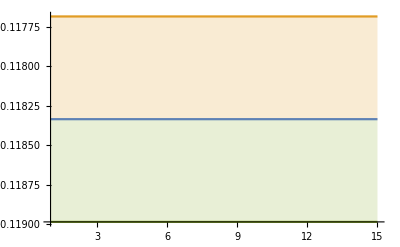

```mathematica
Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,15},Filling->{3->{1},2->{1}}]
```

```mathematica
SpoilHWFLOPlotN3=Show[Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,Length[meanErr2[[5]]]},Filling->{3->{1},2->{1}},PlotRange->{0,-.2}],ListPlot[{Table[{τSteps[[1,i]],meanErr2[[1,i]]},{i,1,Length[meanErr2[[1]]]}],Table[{τSteps[[2,i]],meanErr2[[2,i]]},{i,1,Length[meanErr2[[2]]]}],Table[{τSteps[[3,i]],meanErr2[[3,i]]},{i,1,Length[meanErr2[[3]]]}],Table[{τSteps[[4,i]],meanErr2[[4,i]]},{i,1,Length[meanErr2[[4]]]}],Table[{τSteps[[5,i]],meanErr2[[5,i]]},{i,1,Length[meanErr2[[5]]]}]},PlotRange->{-.03,-0.005},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]],markerlist[[4]],markerlist[[5]]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]},PlotStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau_{\\text{steps}}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3(\\text{NNLO})",Magnification->1.2]]
```

-Graphics-

### a=0.4 dτ=0.2

#### QCD LO - HWF

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={430,430,430,430,430};
NWalkers=200;
Nf4α1LoopBig={0.4,0.4,0.4,0.4,0.4};
aList={1,2,3,4,5};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
csvData=Table[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"],{xx,1,Length[aList]}]
```

({mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.07596541373089014, -0.07591961547197891, -0.07581978963168441, -0.07594101777237273, -0.0759034194747049, -0.07586643294012221, -0.07595056613482741, -0.07605122286451758, -0.07600551295727803, -0.07587994150802557, -0.07593590911842746, -0.07589000315076821, -0.07582793916358664, -0.07591420236579945, -0.07589198800865421, -0.0758788284792071, -0.07592833293510026, -0.07588851854462249, -0.07597458831757795, -0.07605392361295728, -0.07599859716619194, -0.0759271523766691, -0.0759828828252292, -0.07601219311512393, -0.07596271468920142, -0.07606363603866541, -0.07622489489360751, -0.0763429866092387, -0.07624662532583333, -0.07608586063980928, -0.0761659326772016, -0.07615492787223747, -0.07610495468114604, -0.07604938135056366, -0.07603686972985244, -0.07599375903288183, -0.07588140014647832, -0.07587334378093032, -0.07588102927373322, -0.07593107459382871, -0.07601044464242485, -0.07604658831189277, -0.0760387626656112, -0.07591912335622203, -0.07599446268129965, -0.07589027009253178, -0.07597005947225348, -0.07592859045080863, -0.07580957744600841, -0.0758113224314644, -0.07579015491118857, -0.07579527026492246, -0.07581673247542822, -0.07596207796028559, -0.07585519543274596, -0.07577981005186905, -0.07584969599866921, -0.07582198614624937, -0.07591323049273561, -0.07587491810217607, -0.07597288245512328, -0.0761328354266402, -0.07612220572721796, -0.07605584655686486, -0.0761423639752737, -0.07614222554761764, -0.07615191190286866, -0.07615238606864, -0.07622490122588914, -0.07624479349642996, -0.07628834881413138, -0.0762750469737819, -0.07626501601862176, -0.0762693139221733, -0.07625845784925446, -0.07630656599092842, -0.0763478181169777, -0.07625287712844105, -0.07619860524108614, -0.07611561722202348, -0.07608529266963679, -0.07600285086019429, -0.07599994617238053, -0.07587377497287892, -0.0760257441102825, -0.07610586485402904, -0.07628215939627866, -0.07625731419485389, -0.07622893085966258, -0.07624552212792716, -0.07620169707838984, -0.07623988297673401, -0.07620741214308556, -0.07608070665188706, -0.0760361814647469, -0.07603935902661797, -0.07600102480084897, -0.07606066840769851, -0.07610836797013258, -0.07613202326946991, -0.07604020637668485, -0.0759674982262111, -0.07591981740093648, -0.07591808074313851, -0.07589206212191796, -0.07598767075002061, -0.07619642860775108, -0.07609965786387732, -0.07608229017441302, -0.0761953151420809, -0.07602412866552467, -0.07626955166114947, -0.07629328813589419, -0.07622434904893931, -0.07621045144290989, -0.07622977856219208, -0.07618074336629733, -0.07629044489107398, -0.07613473554385365, -0.0763112981121015, -0.07629784518174978, -0.07634650400283441, -0.07633220768310424, -0.07631651440735232, -0.07621537809953928, -0.07631223640664257, -0.07639105180110509, -0.07626683408543655, -0.07640872895812846, -0.0764301019908393, -0.07638292797265757, -0.07625998959062506, -0.07627439191780173, -0.07633823155865709, -0.07636746152502082, -0.07629348910461645, -0.0763431191814842, -0.07636720328363393, -0.07617682054161427, -0.07602913440107369, -0.07595005419428942, -0.07600843192564187, -0.07619502713583334, -0.07632930739301731, -0.07630751884828438, -0.07611349286716138, -0.07604080766121067, -0.07609144678469251, -0.07610690105374779, -0.07604668608790423, -0.07605769080907496, -0.07611139097721566, -0.07603242353378672, -0.07603080409750566, -0.07589915823565539, -0.07579141745717008, -0.07573669365907522, -0.07564655702030587, -0.07588434978899244, -0.0759866167548628, -0.07595829928036045, -0.07578247681190968, -0.07579746811871259, -0.07577002195565254, -0.07596005684121024, -0.07606184508320002, -0.07606189549727857, -0.07606992736021033, -0.07604025587877035, -0.07606770979086405, -0.07606712338811543, -0.07609772019309798, -0.07619201942976435, -0.07607158504659894, -0.07604238515364525, -0.07591253762996987, -0.07604166264368868, -0.07624036285066006, -0.07628711549484207, -0.07617859563097314, -0.0762834484720083, -0.07630311466890763, -0.07628858919422266, -0.07635184955472911, -0.07634756802698439, -0.07617890980075533, -0.07635358351780056, -0.07627108754391586, -0.07628957633273983, -0.07645783146101752, -0.0764444344591897, -0.07625627672576786, -0.0761384116901619, -0.07620836379213448, -0.07606793562826808, -0.07622865702095762, -0.07624887680989095, -0.07604018500306446, -0.07605090481582961, -0.07621090775403812, -0.07635655654530903, -0.0764008954783349, -0.07635467035488314, -0.07630632217503995, -0.07622864677667453, -0.07628762369991812, -0.07633515505511981, -0.07633028099977007, -0.07621706910598029, -0.07627914838987523, -0.07611786649209017, -0.0760670853277089, -0.07624195658267004, -0.07613701954205693, -0.07634296158702818, -0.07633446407048071, -0.07627199443761258],[0.00018688026201120063, 0.0001891219610088073, 0.00019620933478006926, 0.00019746812566637234, 0.00019771878423334823, 0.00018828016747839482, 0.00018908242889033766, 0.00018603676498088405, 0.0001841095892752252, 0.00018877406920575382, 0.00019535291334310108, 0.00020040233487456124, 0.00020571590328442562, 0.00019596257870965492, 0.0002139577218398531, 0.0002073832180479653, 0.00018993995611970934, 0.00019454083969852284, 0.0001933698928994644, 0.00018655143470780767, 0.00018680521118280547, 0.0001783243729526186, 0.00017456220304598054, 0.00018510957930061952, 0.00016906085328127418, 0.00017362492820141093, 0.00017598897303102787, 0.00016137613371167983, 0.0001571417903236154, 0.00016434737092805207, 0.00017879306017451674, 0.00017899053869526485, 0.00017957815063768663, 0.0001797487386075519, 0.00017944977350351236, 0.00017926114098607072, 0.00017306638358720257, 0.0001755462592871505, 0.00018176447375436305, 0.00017280205687995466, 0.000198992030366274, 0.00018464466900442995, 0.0001955556560971391, 0.00020644209934195248, 0.00020609197879574865, 0.00020110532216605835, 0.00021304825822445614, 0.00020970433816995068, 0.00020354751878740973, 0.0002052798502243241, 0.00018173830366749396, 0.00018104175362885944, 0.00017172311204919892, 0.00016779590917104136, 0.00015782534865717486, 0.00016240976665093403, 0.000159578016728706, 0.00015896903831682762, 0.0001586503268927292, 0.00016377748651507837, 0.00016081675131439455, 0.00016316142524373922, 0.00016423707605352114, 0.00015434075076593384, 0.0001749264764455802, 0.00017109725698316166, 0.0001741586311084966, 0.00017668395673047367, 0.0001823377231747293, 0.00017733640392491885, 0.00019158193118613723, 0.00018847372411664393, 0.0001914551416890421, 0.00020661734063559604, 0.00020480018404727494, 0.00019872477812786813, 0.000188706860894749, 0.00020051696838142673, 0.00019828671386486318, 0.00020404289383114095, 0.00019633538209232288, 0.00021311479045337664, 0.00021221422889363564, 0.00022491618636485803, 0.00024673618606308644, 0.0002683079186139095, 0.00022964629804732788, 0.0002338465355437824, 0.00022311428060152076, 0.00021520173510712617, 0.00022599811000895538, 0.00021804521231129505, 0.00023172540098666136, 0.00023137726493094586, 0.00020945229412036335, 0.00021425372929671804, 0.00021806225165167925, 0.00020438838192201288, 0.0002004910752676732, 0.00020243837375058293, 0.00020725100146376903, 0.0002149888166406244, 0.0002100163289922004, 0.00020257867761186562, 0.00019683332642049522, 0.00018685401704049133, 0.00018123575571784556, 0.0001961937290085094, 0.00020973035606542187, 0.00017937883153424804, 0.0001894460620810457, 0.0001930551544321137, 0.00021013161933070094, 0.00020567328013726397, 0.0002179444421879253, 0.0001920796666470539, 0.00018282078866168683, 0.0001782902465908473, 0.00017018299637857733, 0.00018761299926665535, 0.00018373574458634373, 0.0001765776502819943, 0.00018115995706825312, 0.00019961680382708937, 0.00020520249810337263, 0.00019909649617991904, 0.00020028459912088478, 0.000187185871794503, 0.0001993738936275228, 0.00022327571461188528, 0.0002014051707626137, 0.0002158783034622225, 0.00021140091587672325, 0.00019857923857339528, 0.00020545813334888074, 0.00020261720589956635, 0.00020842119501932282, 0.00021745527969674916, 0.0002311426169325868, 0.00022850322108549815, 0.00022895661791051585, 0.00022691625736060624, 0.00023111825934247652, 0.00022255733506185488, 0.00022011365117284747, 0.00024801173079842424, 0.00025380842204953676, 0.00023566111526289658, 0.00022463452937200218, 0.0002165863392676856, 0.00020667641658321528, 0.0002175785643700745, 0.0002173807391650935, 0.00019964029333929776, 0.00020112198720469444, 0.00021196848723010513, 0.00022453767634203535, 0.00021307217702617705, 0.00019675786749454933, 0.0001907664823355592, 0.00019235230007987874, 0.0002066137310417952, 0.00020313092905206286, 0.00020775997614251482, 0.00021670785435580004, 0.0002103950759421865, 0.00020240063060021892, 0.00019457009957492342, 0.00019309388935078052, 0.00018097970106708427, 0.0002165324445333748, 0.00020283250113876795, 0.00020319648223425537, 0.00020591355100760443, 0.00020495476593794962, 0.0002050277501234565, 0.00020467345575791963, 0.0002011714340169579, 0.00020904843782261124, 0.00021190999251254078, 0.00021709058596169775, 0.0002083494446831342, 0.00021401347636835474, 0.0002016111014028046, 0.0002013931074000366, 0.00020934717784044417, 0.00019560819451202823, 0.00020103127379974303, 0.00019906927212808655, 0.00021179208000523717, 0.0002149834017458492, 0.0002309276885794538, 0.00020984548623897205, 0.0002132289263108225, 0.00021584407172062852, 0.00023233562031991188, 0.00024042610199584037, 0.00023112809707211268, 0.00022154969850158752, 0.00020703158422502807, 0.00020966157186431264, 0.00021573339137155546, 0.00021478331215940119, 0.00022482409246895167, 0.00023729911637003842, 0.00022210097874299413, 0.0002235680927254417, 0.00021733439159436538, 0.00019989860149438916, 0.00020046959428901394, 0.0002065218827281602, 0.00021150165026407596, 0.00020145854027660775, 0.0002048196709280187, 0.00022472757226220662, 0.00022960153551586604, 0.00021863242545863047],-0.0761121,0.0000347226,2.38103}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.056974006153863874, -0.056775384051905846, -0.057593163867654645, -0.059053340783944225, -0.06020803290566647, -0.05918887313388613, -0.059463335680710064, -0.058723357459605934, -0.058219655486268576, -0.05677536983497551, -0.056515751766161984, -0.05651201520497978, -0.05622433213704227, -0.05659381853922874, -0.056233486004643965, -0.05648034578916046, -0.056722087267607406, -0.056991131128382354, -0.05734089299674825, -0.05831471491984427, -0.0574797624045109, -0.05773422046270046, -0.05854890000409694, -0.05879959859118027, -0.05787560839538194, -0.06006643859330224, -0.059078209330864245, -0.05915838907860894, -0.05764909207510685, -0.057628086915865906, -0.0571038639442474, -0.05698667673032746, -0.05696385188928453, -0.05712409870205039, -0.05835266430282213, -0.057803896790819924, -0.05809011217849075, -0.057498029741060296, -0.05858808875237572, -0.05870309278613788, -0.059783848605758486, -0.05894588155243827, -0.05855292299757448, -0.05852592286854205, -0.05883365047391066, -0.05917919124968299, -0.05874560503530919, -0.05916322895453911, -0.061156673849146546, -0.05945436559745296, -0.061307817126817446, -0.06068324604338942, -0.07022058306342116, -0.06616764841533546, -0.0634447776115575, -0.06224800941950284, -0.06284422492514949, -0.06604695394155678, -0.06300122310704752, -0.06067803081001702, -0.06030332728703759, -0.061774215862907246, -0.060749002951386334, -0.058717606975852196, -0.05939457420532998, -0.058875360547205706, -0.061565766420972445, -0.06376295576350448, -0.06095859850458591, -0.06133208474650194, -0.05859749152962947, -0.05959203144994072, -0.05769427638199498, -0.057579435248467585, -0.05753658280550652, -0.0572828257899547, -0.056594184984529554, -0.056833176350079444, -0.05672981093020991, -0.057386807764174444, -0.057375199569086884, -0.0571036645841784, -0.05701560078392285, -0.0570611710516387, -0.0569737836879105, -0.0572579131108663, -0.058081905038426966, -0.05825277485441634, -0.057568114869010464, -0.05851473898359967, -0.05857439994699238, -0.05839450026862336, -0.05890842808408043, -0.05910354132435264, -0.05855140864755814, -0.059032804770524624, -0.05841437745373857, -0.05826714844748833, -0.05926302107773842, -0.059440240564668685, -0.060532044799386994, -0.06137410789693414, -0.061151147766768554, -0.06352908757056222, -0.06036212191140712, -0.05925379253350495, -0.059488579252122226, -0.059365328033743454, -0.06049764713352402, -0.06027318058700643, -0.060368531429829564, -0.05965643792417664, -0.059568702737852766, -0.06348672687015286, -0.058379292066265596, -0.05803078972581784, -0.058909158307600344, -0.059462689742517866, -0.05834998118226004, -0.0582547095856578, -0.05899436952323471, -0.05866969493712188, -0.058720733043772844, -0.05964882682198486, -0.05931434079517464, -0.058767198200989655, -0.057861215993424336, -0.05916058411754282, -0.05961560956399129, -0.058578194063786705, -0.05827767093639962, -0.058648345662292295, -0.058592587851171704, -0.0588951249543359, -0.059740299438516546, -0.06058401766069235, -0.059609701711690354, -0.05972163066290145, -0.05992403350552558, -0.06005236908864344, -0.05966011426299766, -0.059820532702353976, -0.05966499649821446, -0.06101268571182885, -0.0606856027735887, -0.061400283641886974, -0.06097503439428445, -0.062354030467254, -0.06141035111337511, -0.06182281498331873, -0.06261486598440931, -0.06187142771432764, -0.060865462291241505, -0.06048080208276365, -0.061218700341649626, -0.061071125612349134, -0.06139606497062329, -0.07847571207926558, -0.06223111974322468, -0.06261602784102743, -0.06301885091871132, -0.06321245147834928, -0.06216653248996035, -0.06148950616253717, -0.06338095160621096, -0.06816258121804379, -0.06318761864206807, -0.06402422492609118, -0.06408222977216282, -0.0642170206003495, -0.06582956755912679, -0.06883723935635523, -0.06805646617071419, -0.0695885843380686, -0.06755776025434924, -0.07047067810756603, -0.06721522979464972, -0.06902339021791135, -0.06735000190500554, -0.06575447460657348, -0.06636715383391474, -0.06571343409501909, -0.06673017426664057, -0.06666260983008265, -0.06616265116581849, -0.06645519882263637, -0.06774599450575758, -0.06687450284517184, -0.07070116823947714, -0.06825115671852405, -0.06643363805064559, -0.06668511571038988, -0.06595376442424278, -0.06819674415916106, -0.06922171202390773, -0.06926610338414196, -0.067885353431062, -0.06804542340191945, -0.0681705101868988, -0.06830254072761235, -0.06861066939582561, -0.06793272069836905, -0.06820564016170462, -0.06728289823986439, -0.06732326954856493, -0.0673486274268228, -0.06795929141024878, -0.06870351047410311, -0.06836846010571465, -0.06915761224323946, -0.07138828238646144, -0.07320910705981958, -0.07064616968051067, -0.07150936598097601, -0.0736335917622122, -0.07113048450531742, -0.06913322742113528, -0.069365253501277, -0.06795473710466775, -0.06911572712458378, -0.06839383507137663, -0.0691498635005977, -0.06906696093375275, -0.06963179095628669, -0.06981865055002848, -0.06968401427065743, -0.06918758908563533, -0.06906110418653578, -0.06766998998475857, -0.06829518883331674, -0.07008451545991602, -0.06926634845623329, -0.07382120980080084, -0.07695607295661351, -0.07290972298070655, -0.06810365793453073, -0.06867391611824006, -0.07267113510525475, -0.06736232226097248, -0.06664147378345085, -0.06676278555622342, -0.06763764272336754, -0.06732272620422397, -0.0680767801079977, -0.06741086089841565, -0.06848577178635572, -0.0679431170945941, -0.0662060567118225, -0.06585574407817261, -0.06724973539034468, -0.06834219182664365, -0.06731694522036885, -0.07157448844786117, -0.07807120256011499, -0.07427758015889667, -0.0755668210507586, -0.07243836465737519, -0.08523799495084017, -0.07629093440109964, -0.07094853791128906, -0.07010355495080195, -0.07058732632075157, -0.07464842528999581, -0.07287389550033897, -0.07280333709480691, -0.06930944536923685, -0.06930647044838469, -0.06824136251917912, -0.07032963705240176, -0.06816978308052918, -0.06901753526413684, -0.06889716810589973, -0.06831752555807008, -0.06703566613303594, -0.06710974077385527, -0.0670928133278064, -0.06681331381093751, -0.06669778719764383, -0.06627429346815089, -0.06625514015768583, -0.06754007093148585, -0.06998057716800678, -0.08494441254397136, -0.07466563629565115, -0.07365161871040718, -0.06973252070100897, -0.07140965310006504, -0.06934313730820157, -0.06747954385530265, -0.06676575787655106, -0.06613749521638208, -0.0655589303838165, -0.06544007650766412, -0.06492585331764257, -0.06581146339872766, -0.0665113936430973, -0.06574978562737166, -0.06601555955891412, -0.06526587871128227, -0.06450855807581511, -0.06475338410388788, -0.06583168934051191, -0.06517897754488179, -0.06553448862078953, -0.06467981176782708, -0.06724012540382153, -0.06969806698314061, -0.06826581741857335, -0.06827933563605632, -0.07343546802004611, -0.0704222924296187, -0.07604700241602134, -0.06749048049521703, -0.06644670479014184, -0.0673043274571289, -0.06660492890477013, -0.06563646390631354, -0.06595172948450122, -0.06534585153867313, -0.06637098795671544, -0.07043869390606923, -0.07325201473195607, -0.06499817315387652, -0.07011887388032167, -0.06935574446612347, -0.06736689764401665, -0.07028324173289943, -0.06673749376781203, -0.06721644355072853, -0.06642780240074202, -0.06793945731992014, -0.06681776966424616, -0.06829878975987645, -0.06845212233163812, -0.07099586328918724, -0.07022032971537641, -0.0677186857333318, -0.06671795701351863, -0.06645023794343885, -0.07292810987603887, -0.0676581825343183, -0.09811417053379094, -0.07018983467898926, -0.06944026846403702, -0.06692826077540333, -0.06590501200931868, -0.06545155557457162, -0.06536805331542628, -0.06629058323174376, -0.06565077567594345, -0.0666263666131523, -0.06783423622209311, -0.06839757924689654, -0.07044425583552417, -0.06954807437145621, -0.06861465390901503, -0.0696995619628048, -0.06992972246683526, -0.06906370090742099, -0.07163756097673382, -0.07049361309813726, -0.07128189068227901, -0.07071172716400555, -0.0715663497333192, -0.07084781097129754, -0.07007096870837831, -0.07096988955763156, -0.07083069789794696, -0.07346071664223293, -0.07114707294885309, -0.06967795484386372, -0.06880957848878724, -0.07011945727814962, -0.0700798424043549, -0.07276387571097018, -0.07052844207689468, -0.06931690254256917, -0.06926816115572344, -0.07034532175472406, -0.07171777136447392, -0.07232910511035859, -0.07356722704894629, -0.07265376503939378, -0.07139498041282501, -0.0739866478507897, -0.07314840367254327, -0.07474929564838591],[0.0012829873706722383, 0.0012989365305518137, 0.0015984035778738954, 0.002044873550145068, 0.00240149533893118, 0.0020211754929269194, 0.001978183329408273, 0.0017568526605776103, 0.0016014187189812192, 0.001301825918005332, 0.0012116791228307955, 0.001178192050772632, 0.0011237103222061615, 0.0012049174570046414, 0.0011662910642679819, 0.0012444281462057082, 0.0012664329953144455, 0.0013436745725497977, 0.0014338160087299188, 0.0017609210913185013, 0.0014143632744465513, 0.0014865000220669632, 0.0019499602587445821, 0.0020322819830934195, 0.001705692288866745, 0.002978359136987281, 0.00219912452817932, 0.0023737116062084234, 0.001635155006059453, 0.0015890351591221537, 0.0014171006798506846, 0.0014203836998171807, 0.0014681112510388599, 0.0014862300644552205, 0.001849064515811285, 0.0016854655029772665, 0.0018011191088305768, 0.0017298044641510168, 0.0022011170957383017, 0.002213808557629005, 0.0031473408662489946, 0.0025377909322134382, 0.0023360312664691156, 0.002310436218493982, 0.0024273346263840997, 0.002822207149634219, 0.0025376976032564225, 0.0024237587687202648, 0.004521670473284499, 0.0032242927550128267, 0.005133027661033696, 0.004436589659229103, 0.014485510112061019, 0.009910458201352562, 0.006473648053684121, 0.005483911432652311, 0.006124082599849166, 0.00915695760933968, 0.005779536049082377, 0.004267240483697186, 0.0042738896096565955, 0.005696002493201319, 0.004401548759393395, 0.0030283336823307013, 0.0033649874567075735, 0.003490954555398316, 0.0055140956363219674, 0.007591961109286058, 0.005037320409343654, 0.005485811340069825, 0.0030491453036706096, 0.003201725094352188, 0.002083542419539453, 0.00200679994351294, 0.002034569451851914, 0.001896655298282198, 0.0015134786180720317, 0.001700163828582605, 0.0017263865057732205, 0.002044761892716094, 0.0021620010420168, 0.001870449095890484, 0.0020145320033453625, 0.002027644568660814, 0.0023684760208511533, 0.0024786801735921767, 0.002742119728498172, 0.002915724117739626, 0.002439583287020646, 0.0029949848184805503, 0.0029117917192495665, 0.002682205501313932, 0.0026070834333468303, 0.0026004320347344312, 0.002422262091476933, 0.0024265188420216463, 0.0022706726589022163, 0.002132982533143929, 0.00252477230936116, 0.0027956196811882755, 0.003457047015969107, 0.0032857339815224253, 0.003379859687297506, 0.004818442096526374, 0.002779260441082472, 0.002236720869249664, 0.002229416195508304, 0.002079796952885801, 0.002420285818495462, 0.002325615846838394, 0.002364113152456317, 0.0020996467429891773, 0.0022663506472739695, 0.0063915041263330925, 0.0017926544244167555, 0.0016594214596286694, 0.0020003425995621924, 0.0022654579086323207, 0.001656782993596044, 0.001593548751178805, 0.0017364334142477486, 0.0015847892464374105, 0.0016397037393811988, 0.001978818501706707, 0.0020411971449538387, 0.002097232854073705, 0.0019610594312212595, 0.0022582089267598657, 0.0023546345165311763, 0.0018451533433621198, 0.0015516061211094249, 0.0015977655432843328, 0.0015498613631187703, 0.001588829287587836, 0.001794205806729952, 0.002011747787690901, 0.0014151700050798071, 0.0017558819696640836, 0.0023635139579416702, 0.0023294745034312197, 0.0017269523515460405, 0.0016151317404123186, 0.0014453329108593679, 0.0017780757707241556, 0.0016823373447462967, 0.0018582984335384748, 0.0018265363246435932, 0.002302840827760262, 0.001703784463154622, 0.0017406120233064845, 0.0022718835444879813, 0.001956789361913724, 0.0016443741499482655, 0.0014821043072904619, 0.0016235752917446633, 0.0016828156159515864, 0.001698683792976526, 0.01697044402319223, 0.0021224237939477973, 0.0021484522295327456, 0.00235986991120967, 0.002605794771274175, 0.0018134031621232808, 0.0017667721164291302, 0.0025441279299187065, 0.006128394992040049, 0.0024549323929459466, 0.002536827351310886, 0.0025941674404854438, 0.002499017903372452, 0.003379062210125778, 0.004510864378738295, 0.0035797511149486473, 0.004193903631789702, 0.0031865650107510534, 0.003935261277327046, 0.0032721463063340762, 0.004620936458355249, 0.0030464403349837192, 0.0023303695908739722, 0.002494051478070221, 0.0020953305697345697, 0.002319283673285259, 0.0023709726235731166, 0.0024441871450632297, 0.0023328905646404874, 0.0026420051189349866, 0.0025733041323181645, 0.005112644713430903, 0.0033486719778189162, 0.0027102055734533545, 0.002699297695461491, 0.002393622815400136, 0.0035634820894414154, 0.0038089082816649524, 0.004009708059019358, 0.003872376070136103, 0.0039453332568674905, 0.004234924129865995, 0.0036522299369993465, 0.0036169731362103922, 0.0030721771592802623, 0.003383722364235486, 0.002572351663128292, 0.002789863363572304, 0.002563595036467167, 0.0026493917168863624, 0.0028390050198045594, 0.0027406237034246707, 0.004322955449731848, 0.00563062011301121, 0.006719716221990897, 0.003610747438173328, 0.0041132646823286104, 0.004668932104925027, 0.003184706141731273, 0.00266349239258884, 0.0027971545331021965, 0.002233261621182066, 0.002403733686272988, 0.0022996764342334023, 0.002402768900590501, 0.0023580595655058414, 0.002673396930700566, 0.002720437343416466, 0.0027483418041967587, 0.0027151612593064468, 0.00256893765666928, 0.0022915018056512406, 0.0028257275483560976, 0.0032081556728403068, 0.002912661772245, 0.005346126316836667, 0.008416705200919888, 0.005129820770926728, 0.003166965992251535, 0.0035172884158169806, 0.00677675742925352, 0.003105941223450146, 0.0026645977048228237, 0.0029224675845090317, 0.0037790811082507574, 0.003326284563729245, 0.0036391103151451414, 0.003571544328439652, 0.004147320045388078, 0.0033635760850288777, 0.0026345368190698265, 0.002760490415928719, 0.003250529602617758, 0.004526140765906207, 0.003038105469917825, 0.00537766659751547, 0.011389899185978844, 0.007918718790289941, 0.00854500731181283, 0.007199703823549282, 0.016919778839329467, 0.009373480756484448, 0.00501634228458133, 0.00456414342634558, 0.0045529488717595675, 0.006736360271600709, 0.005339344450834313, 0.006453878462231157, 0.0035690763386912994, 0.004363092865036191, 0.003858721099571001, 0.006082030275644714, 0.004326872823724183, 0.004782872478975377, 0.0044797070174455245, 0.0040505022666371395, 0.0032353854327458876, 0.003134102304850928, 0.002789586483323889, 0.0027241782314262495, 0.0027939604665116195, 0.0030376998932012816, 0.0029600486847446606, 0.0038310199450636933, 0.005786110236171987, 0.018538017775027366, 0.010093471716686774, 0.009623845012798275, 0.006428766608551453, 0.007560506867505958, 0.0054010706568788334, 0.003584677805499499, 0.00336085185901539, 0.0029689727493890615, 0.002933155809724273, 0.0027889679958802284, 0.0026066816641978972, 0.002910510607760061, 0.0033943641212864405, 0.002943279569098429, 0.002845127515185762, 0.0027456221773522562, 0.002221417030472219, 0.002287473481872675, 0.0027200689241147612, 0.0024252529902409085, 0.002241121262404206, 0.0019138382348474526, 0.002857567804061164, 0.004363489236270105, 0.003914682454457886, 0.003964332525164858, 0.008305355368573776, 0.005473422257381692, 0.011657126854323682, 0.0027805719164551343, 0.0026106100405962444, 0.0031001472434774606, 0.0028154079919540604, 0.0023169390112370183, 0.0022712713620466, 0.0022222535087598537, 0.0030858675470132944, 0.005363807905024882, 0.007643456384516074, 0.0022821450573360705, 0.004956545273516601, 0.0037735893892499933, 0.0029465761440435555, 0.004964057628257758, 0.0023958769905450617, 0.0026208990642856184, 0.0023596851603710205, 0.0031282931456466444, 0.002464014155127506, 0.0034082792405789437, 0.003281894971384955, 0.005178502659522288, 0.003977458850055467, 0.0029111389464262245, 0.0027984256753345016, 0.0028066067592387657, 0.007279376828584036, 0.003424631296126286, 0.033421475268349994, 0.005736402287298546, 0.004573785904742693, 0.0033760555819191867, 0.0030644479844880645, 0.00283453376955369, 0.002670213186930073, 0.003014028538981992, 0.0029505499883202566, 0.0033114334532104044, 0.003879530292004219, 0.004059648342515447, 0.005209622053510183, 0.004372420853996512, 0.0037427206971138985, 0.004258757289354458, 0.0044575014087968445, 0.004288556285998401, 0.005377247275538037, 0.004653752450125202, 0.004947024618030232, 0.004901715400664472, 0.00553583119440978, 0.005101410333998104, 0.004255162060628832, 0.005014895887461533, 0.0054095822748455894, 0.006931345499989449, 0.0055011937029917825, 0.004359215681849875, 0.00393232338638509, 0.003972861428074488, 0.004062702249281475, 0.005228916454759909, 0.0035524425412913137, 0.002962968899288282, 0.002840201688362141, 0.003190608697751311, 0.003457376285279681, 0.003779746775717651, 0.004384410573722007, 0.004302808703602423, 0.003987890946154092, 0.00475760803042045, 0.004571665721768606, 0.004826564189798201],-0.0580098,0.000477414,0.502067}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.045612558888762894, -0.04560917657072649, -0.04486279722826777, -0.045447014389643076, -0.04583861648368492, -0.046558548193253425, -0.04597911131447267, -0.04577644703815697, -0.04697493239871723, -0.04560756099307158, -0.04470820081464392, -0.04532649582722837, -0.04539277571628667, -0.04611338823681879, -0.04569724519892796, -0.045793350751722056, -0.04614126701099321, -0.04590072106647264, -0.046105825725481824, -0.04750552120888664, -0.04703027620268904, -0.049292799873632415, -0.04728088634552355, -0.047464148631404406, -0.04690247314901137, -0.04599109139068944, -0.04708682558054064, -0.04646580986327204, -0.04714076866179592, -0.046131785364563284, -0.04692321660700277, -0.04592679692562311, -0.04573635083741819, -0.045094877589990465, -0.04623012085345234, -0.044469434512078874, -0.04478036962297486, -0.04446682803434125, -0.044542370299570394, -0.04436346146032874, -0.04419584714050411, -0.04394330202044391, -0.0441811366596703, -0.04403438166057667, -0.04393192700293412, -0.04382934447107872, -0.04405297774092949, -0.044417023528456584, -0.04406517477735229, -0.04385405339876704, -0.04367459715232789, -0.04348981223988353, -0.04312235410480322, -0.0433696168873682, -0.043517590451712385, -0.04355111752501519, -0.04364508938902887, -0.04376910646973328, -0.04409101152086982, -0.04385355779687085, -0.04403899595873457, -0.04370005895961564, -0.04380338950731869, -0.04357773634868937, -0.04353726533056552, -0.04357220308434893, -0.04399407049272535, -0.044177332049909965, -0.04486212842579987, -0.045226085300725805, -0.04530792206655342, -0.04685807843529935, -0.04677931641009516, -0.04566414220012048, -0.045984607114592256, -0.04569905182409844, -0.04643474227183254, -0.04609103817680242, -0.04556628979857121, -0.04652159395108596, -0.046648120295435865, -0.0457747134807421, -0.045406492218954965, -0.045590359571999944, -0.045812077286666086, -0.04615858302192427, -0.046647078840354746, -0.046494693914416185, -0.04642451336848303, -0.04657954202951411, -0.04758502151828695, -0.04734991895247465, -0.04663656560161996, -0.04693244248918746, -0.04700170591754242, -0.04703367281894781, -0.046216349532557544, -0.04669610134493025, -0.04686541682210722, -0.04713022351941272, -0.04712520730235564, -0.04742865396625001, -0.04696750416765594, -0.04707261896380689, -0.04675488412277739, -0.046930225363355775, -0.0474872438543503, -0.04678884076216782, -0.046822069848817024, -0.0471707273233102, -0.047458725530207344, -0.047782488285627686, -0.04956563782344539, -0.047954074997044585, -0.04914833291038496, -0.04862438310898013, -0.04987079058884602, -0.049215275187204865, -0.04991545695425749, -0.04933827021820708, -0.049469671438385786, -0.048465332953980624, -0.04756097535847679, -0.047293562739120325, -0.04709114919410773, -0.04649036865978689, -0.04638571424104016, -0.04701228177592493, -0.04721305854392882, -0.04718644342669414, -0.04740995617922706, -0.04846639731123415, -0.05051210229062359, -0.04788096477396084, -0.0497596580293143, -0.05030016016929114, -0.051915451941459835, -0.04838215519853848, -0.047640489618909106, -0.04771024647167507, -0.04967336414653784, -0.04882481112478744, -0.04823128681057897, -0.0482876124982893, -0.048590312412855795, -0.04930781398406621, -0.04812495372159232, -0.0495371493084768, -0.05139807931392534, -0.0509402126426473, -0.04913187214499297, -0.05017603568972383, -0.05310229772660007, -0.049903137207019214, -0.05057244774286215, -0.05173945878408293, -0.0510614543186007, -0.050889672280654705, -0.05141022244381792, -0.056366250068605635, -0.05200482574321912, -0.05305915945627796, -0.05331830237254759, -0.05276530355120823, -0.05379527536431321, -0.053138767913912685, -0.05214145053653489, -0.052632983493727595, -0.05244554463845786, -0.05276801762103268, -0.053415038010626165, -0.05462647459384543, -0.053029124385149215, -0.0532057951039009, -0.055782270776250586, -0.05425610059832395, -0.05415170785217523, -0.0535173233855734, -0.05350866578538371, -0.05914023750299016, -0.055145398373838125, -0.05524832797814255, -0.05293950865276763, -0.05323885080867222, -0.05378864636249396, -0.053726888439065305, -0.055446483717126384, -0.054120883152568695, -0.05488122228385444, -0.05468297142266402, -0.05415845899854713, -0.05408213379181174, -0.053090460095743544, -0.054341423690698706, -0.05576976229389953, -0.05661596828185969, -0.0577794023067, -0.05604769770817783, -0.057566494653709235, -0.059860214642865395, -0.06010431075333302, -0.0556227534712569, -0.057054172363442714, -0.05737012658341667, -0.0543318694573831, -0.055170069426604525, -0.05529666128138053, -0.05546770008458589, -0.055351554730643654, -0.054725456061868065, -0.05412232482817846, -0.054790389362977004, -0.05465800880986633, -0.05490261215787294, -0.05521478144460555, -0.055371546070608735, -0.05486565518343426, -0.05805710760699417, -0.0627172239538822, -0.06692428946720229, -0.06412049677024083, -0.0648872425818413, -0.07396752685095642, -0.06398036093556723, -0.06544673197673379, -0.062335717302009076, -0.06017817283353703, -0.06082646427813083, -0.05906149408136097, -0.05907122792670423, -0.05998886523625088, -0.058809661073606884, -0.05868476437577854, -0.060733473753591095, -0.060904755901976755, -0.06410216379126936, -0.06500220666692268, -0.06876411737737444, -0.0654352212219085, -0.07534447235039571, -0.06732427679542109, -0.06447328635944752, -0.06359993521773614, -0.06412959157732458, -0.06522717432658966, -0.07237367568994155, -0.07909729817183099, -0.06688421981870812, -0.06395841376405383, -0.06495912434422678, -0.0643059934363471, -0.06344305198732543, -0.060987249558374354, -0.06684825086700535, -0.06755805211706423, -0.06376494165566167, -0.06442766264718726, -0.06801326415380121, -0.06164428519784523, -0.06028615706034184, -0.05790029101974863, -0.058556692384271865, -0.05774354330609653, -0.057902049819048666, -0.057904331193159124, -0.06077336778364674, -0.06044262219512535, -0.05849606714592082, -0.059698222154983986, -0.06243241146260714, -0.06344962357879669, -0.060885102237478776, -0.06169784067072247, -0.062296905931869095, -0.05972181922695936, -0.058398255403167586, -0.057917810121562815, -0.05849716827287754, -0.056339295278674394, -0.055884126610782514, -0.056157884018482734, -0.056406442333588235, -0.05628037340505564, -0.05675330466162458, -0.056971855812217156, -0.05649460116429214, -0.05571767592462022, -0.05495891760094451, -0.05513503960949359, -0.055038915168202626, -0.054592204124383314, -0.054448100868436426, -0.054454221727903755, -0.05419087616809347, -0.055044696808475686, -0.05556116754115622, -0.05448278385962741, -0.05540128305908178, -0.05410161524215206, -0.05285745801373535, -0.052995974934599926, -0.053610451872834045, -0.05397171313378036, -0.05594020398071097, -0.05478614887453909, -0.06552165918840892, -0.059622525824722564, -0.057622642041215553, -0.05721753672212781, -0.05515332613774428, -0.05474835064028918, -0.054009513560386545, -0.05405773491282293, -0.05320668988876972, -0.05291862136883886, -0.053645075616762586, -0.05395900828873818, -0.052883151493986626, -0.05216269017684964, -0.05112115995172785, -0.05149727040531452, -0.05116294369886449, -0.05234733053782713, -0.0526296172375708, -0.05301028735315363, -0.052811197499769556, -0.052689614092402956, -0.05278055618854402, -0.052889922922384265, -0.05383369019493742, -0.05429226866084038, -0.05354564574103169, -0.05516633017538543, -0.05823539998234251, -0.05820631564539554, -0.059961394108551946, -0.05848890419687765, -0.05892281115481779, -0.05831263270448438, -0.05962075497176574, -0.05834463404535379, -0.05761020383162954, -0.061499659828970106, -0.05959459416884442, -0.061005268192081887, -0.05906755931331962, -0.057039528156560215, -0.05716501738198277, -0.05773247590782718, -0.05781676674616003, -0.05795271942616684, -0.05832166736315032, -0.05928112676069098, -0.062461816341754225, -0.05997952570120059, -0.058882869329229225, -0.060697358239190834, -0.059049968821049376, -0.0588040448126416, -0.06021455343587351, -0.05986496634817596, -0.06062340644983501, -0.061056912711484744, -0.06444393354740613, -0.06549803001056526, -0.06889859210683107, -0.07472741026671544, -0.07071970967503781, -0.07240388072583316, -0.06877919801664181, -0.06470581334820087, -0.06251613006785733, -0.06522585976246237, -0.06423675937537239, -0.06288424472022902, -0.06615611606144645, -0.061628057385765656, -0.06308370196845477, -0.06507286584473489, -0.06331261691519538, -0.06850934793599235, -0.06599396495213115, -0.06604547842039529, -0.06487570202908935, -0.06952417249969069, -0.06980802875096943, -0.06733699658537798],[0.0018452961077714475, 0.001834547951826267, 0.0015876520329326858, 0.001752671449664693, 0.0019243284147615952, 0.0021246211877617616, 0.0018698301336468606, 0.0017503866512211363, 0.002448469607514918, 0.001965145022683856, 0.0015415020041634894, 0.0017756124249649096, 0.0018519945744379933, 0.002097783328199887, 0.0018940311638874364, 0.0018882460193359724, 0.002067936012622287, 0.001973708468667269, 0.00203049116477165, 0.0028948056498510877, 0.0024667759587516385, 0.003998751402550549, 0.0025510322223604074, 0.0027417510126858504, 0.0021959525629833077, 0.0018870794683797916, 0.0023340387484763517, 0.001881739998954618, 0.002523282169572421, 0.0018827996462979575, 0.0023085092569956915, 0.001784015490955169, 0.0017306514928532475, 0.001519182214777696, 0.0024868831044811556, 0.0012951471303141835, 0.0013259656820607563, 0.001290854875784186, 0.0013169456444832583, 0.0012928429775191503, 0.0013124756704152233, 0.0012441924001034036, 0.0013106327663361345, 0.0012685117504791315, 0.0012749464467901315, 0.001236559862775283, 0.0013070725302581317, 0.0013624144901177688, 0.0013619143774020483, 0.0013770507798420253, 0.001292254153025683, 0.0012224496914380624, 0.0012045557320087637, 0.0011737609657289602, 0.0012234907238313738, 0.0012128137358446457, 0.0011980186933510056, 0.0012003745443833803, 0.0012412508090528006, 0.0011780676921918623, 0.0012074003626675065, 0.001141113124829924, 0.0011714740667376853, 0.0011348542298257706, 0.0011348650170806007, 0.0011545065976372839, 0.0012016581601102683, 0.0012558337268421265, 0.001506890342699359, 0.0016300407303106023, 0.0018429188110021474, 0.0029834243654522684, 0.0025281152759039443, 0.0017276709413760942, 0.0017972895878368385, 0.001673209485843946, 0.0019649939919054843, 0.001777757724985107, 0.001665339755678943, 0.0018966167621266576, 0.0019243458927463957, 0.001672499423382096, 0.0015815364525319632, 0.0015658668492256299, 0.0016265413798001263, 0.0016968715680493421, 0.0017906953413041537, 0.0017759751865119326, 0.001793519902542567, 0.0018081908958235892, 0.0022921392409478033, 0.002167818950030122, 0.0019161133525573155, 0.0020325350474489703, 0.0019647792841184035, 0.002087930438022655, 0.0017869432919665796, 0.0018453297840369004, 0.001962798381155607, 0.0018907856840351287, 0.0019270312311149395, 0.002021058426606985, 0.0018797385685927846, 0.0018708172523689323, 0.0019238148763914243, 0.002152168729100023, 0.002452368533157879, 0.0021876486431991462, 0.0021081692143275297, 0.00236802681225052, 0.0024860087108625017, 0.0027932054882972655, 0.004451950528567992, 0.0028518110154704145, 0.0036796283746026565, 0.002827854072632094, 0.003571070766493609, 0.0029431574482301805, 0.0032106513192254444, 0.002981103475732781, 0.003142961995463977, 0.0028301903807989863, 0.0024013687144849084, 0.0023356134544703627, 0.002229602599194327, 0.0020772603504808874, 0.0019630229179119717, 0.002007028154855694, 0.002023841136745326, 0.0019224052597373272, 0.0019119384002924836, 0.0025815551030859384, 0.004056379435356956, 0.002134240184534818, 0.0030927619237811075, 0.00410903636912616, 0.00552161559668535, 0.0025693762067178095, 0.0019605754105346406, 0.002049215904791263, 0.002948939232893745, 0.002390964527209836, 0.0021951648792310333, 0.002017164202774203, 0.0021027124065326743, 0.0023960284815527227, 0.0019481648244000012, 0.002575580636712362, 0.003622615696311306, 0.0032830195926309516, 0.0021680110090570126, 0.0026878366593564764, 0.005228886071565349, 0.0025397320437289634, 0.002641359554010466, 0.003707548490247333, 0.0028685433409955494, 0.0025710157548976082, 0.0028080655468747163, 0.005520335816720001, 0.0031178901374417584, 0.003181372495887261, 0.003256559936627383, 0.0030986508929470163, 0.0031321547170508482, 0.0031010299032736438, 0.0026454414118500355, 0.002789138768030423, 0.0026193053768883753, 0.0026631259228038807, 0.003199064871980448, 0.0035458428521031706, 0.003069933087226326, 0.003029054075013807, 0.003974609259762329, 0.003153418361473503, 0.0031521225878794893, 0.002979041660109227, 0.0031722339130288205, 0.007048159657997956, 0.003531444256741918, 0.0038563073977371416, 0.002602395706916498, 0.002673314158025083, 0.00283809447845926, 0.002789970913484639, 0.0033191943314589073, 0.0029841916631108494, 0.003446300105565861, 0.003391535743595698, 0.0033967006334082537, 0.003470915221297047, 0.0030599337667241446, 0.0034540149564620945, 0.003857736558160241, 0.004273837383599196, 0.005070737085276075, 0.003952757702058964, 0.00522317767767958, 0.007050321845871849, 0.006942572102820757, 0.004102742046851622, 0.004844880122420096, 0.004711506694800947, 0.0031752781763617465, 0.0034743729849186136, 0.003419961228367, 0.0034463605884655674, 0.003378304426650945, 0.003049044671603493, 0.0028370690860712662, 0.003131069275070842, 0.0030631341646112356, 0.0032835199578354147, 0.0032067556380731715, 0.002950734898631854, 0.0027954442716902434, 0.0046187632983519305, 0.007982248731928883, 0.011313677935505539, 0.008333274648168468, 0.008043424154815754, 0.01614112757094738, 0.007585593371050052, 0.008811212024278554, 0.006249721287541332, 0.0049975853615358695, 0.00525069291973651, 0.004797151638266211, 0.004529697270843211, 0.004740300116297124, 0.004234153050403707, 0.004629623456255132, 0.005948244223813985, 0.006226803091385721, 0.008083246012835315, 0.008894325618451703, 0.010423814155188935, 0.00888778220694289, 0.015806919565701915, 0.010042361032482896, 0.00785748676426563, 0.007729000156716439, 0.008130844655050557, 0.008633702796629136, 0.015084515334115624, 0.02029611465607366, 0.010815257359484316, 0.008166161360559065, 0.008782385540243774, 0.00858166473537073, 0.008166585002240751, 0.0064705275626673175, 0.010387488299153558, 0.010864435533676043, 0.008454381957657223, 0.008991261043694899, 0.011618935248626186, 0.006143634980915495, 0.005464276516728521, 0.004069504915359169, 0.004472428278431488, 0.003993940868093635, 0.003996688081805737, 0.004101637606047109, 0.005074979545753908, 0.005520201655812329, 0.004624175408702894, 0.005822405232943172, 0.007973273204586007, 0.008615513229188635, 0.0062819169500169135, 0.006312597972936827, 0.006686481706849703, 0.005186878637706739, 0.0043694824880175145, 0.004341735424269753, 0.004557045797943413, 0.003987546300970958, 0.003916637419389544, 0.0035386655126776476, 0.0036862187515774754, 0.003536422510987632, 0.003668875633137643, 0.004004379342729226, 0.004148222856457221, 0.003754788570913422, 0.003243073770621722, 0.0032021136317306968, 0.0030883660263778027, 0.002838402716857048, 0.0029339688374507484, 0.00299845917271541, 0.0028976114414106325, 0.003258009728192083, 0.0035416650038460435, 0.003264263768199932, 0.0037979893588777876, 0.0031874180799607937, 0.002747571934193158, 0.0025446819071213845, 0.002773950057141173, 0.003369349355590529, 0.004365897385880633, 0.0042675332143808295, 0.013861242451083056, 0.008514243284020671, 0.0065204155606375285, 0.005509009314481336, 0.003752809444880152, 0.003793957173558678, 0.003377690272739859, 0.0035992632801295095, 0.002887307023397732, 0.0030278384071346057, 0.0030011620195574615, 0.0032043237238012154, 0.002722720902455216, 0.0024934872000807657, 0.0022793152645678417, 0.002389776837497887, 0.0022471803358760085, 0.0026791202000123883, 0.0028781966834703567, 0.003079962740198472, 0.0032218616631578207, 0.0031594077752815216, 0.0029184365142272896, 0.003227521662070464, 0.0036338174036799, 0.004294020878312987, 0.003672514952586558, 0.00428479407826088, 0.006345581574941447, 0.006421817070785211, 0.008062295993771939, 0.007020220755449101, 0.007150625752287828, 0.006662081307892375, 0.00776891408111634, 0.006381123263955725, 0.006339181991394975, 0.009254273626897215, 0.007597540678010731, 0.008720612695294573, 0.007052377491943263, 0.005466318212341901, 0.004874068080739313, 0.004764523710310968, 0.004960351377269967, 0.005333724390480228, 0.006018911681001419, 0.006578472614369325, 0.008685632179695266, 0.006795003636999753, 0.006667900986210871, 0.007878229906914183, 0.006738208023960334, 0.006864960936280442, 0.0076364127881407215, 0.007070518584230674, 0.00813443041099042, 0.008562997693069905, 0.010789422804004238, 0.011839000177674941, 0.014735134261344849, 0.019274539941235336, 0.015730246905048872, 0.01640378508053464, 0.014216982421351334, 0.011466976891085823, 0.00990700424052328, 0.011420606643248458, 0.010320381425654777, 0.009506817415013902, 0.011966188935551701, 0.00888392872865266, 0.009863128017334294, 0.011230143417020054, 0.010174430180129534, 0.014493656236957883, 0.012501775894959441, 0.01231089403321257, 0.011225667901950582, 0.014235640362545196, 0.014499342553128186, 0.012431404547381416],-0.0440747,0.000611683,0.268353}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.03555498274894136, -0.03607044776666875, -0.03639346023422973, -0.03640530398850335, -0.03699355210338885, -0.03655171155214037, -0.036674079051163176, -0.036831962240742824, -0.03631466819304263, -0.03605431319162867, -0.03615071363079726, -0.035721174378354655, -0.0355545409667468, -0.035560400724067076, -0.03538691308831256, -0.0355275983887616, -0.03557150513006713, -0.035288435580610476, -0.035458073821981795, -0.03595778372220159, -0.03576694952044951, -0.03596501521612202, -0.0364311468436424, -0.036415933077386387, -0.036133634446726695, -0.03629190902400528, -0.03643435063779925, -0.036499558701138295, -0.036488993052619566, -0.03654814282408008, -0.037173389994738675, -0.03705792408584411, -0.037129561803109334, -0.037398227107864404, -0.03730963978115909, -0.03730589313023162, -0.037131258583608225, -0.03676519678714794, -0.037079967465217294, -0.03724067974532567, -0.03867857497459817, -0.0371855122419367, -0.037465629898524457, -0.037604418492027676, -0.03715224132668014, -0.03757067878047539, -0.03803793193225583, -0.037682164172082144, -0.03729022593459066, -0.0365336991021187, -0.036678441781849876, -0.03663229502716273, -0.03646807505278958, -0.03698837229151883, -0.03717431130539624, -0.037473587781042865, -0.037662696519342356, -0.03737209904383359, -0.03693421269190122, -0.03730930790916069, -0.03742237796940268, -0.037911457161681976, -0.03777335528824939, -0.03732282611192013, -0.036958336958103556, -0.036704062637253156, -0.03775275373974572, -0.03796934830950062, -0.038243981180241866, -0.038689397644685576, -0.039344228636976356, -0.03841003167446218, -0.039405236665861536, -0.03993368367486647, -0.04011742836320846, -0.03986361846527586, -0.03892660144545922, -0.039971576742422785, -0.04000085053904289, -0.04011434992688981, -0.040969513484744015, -0.040636561680593784, -0.04018738276913034, -0.04058217414673078, -0.04119998086104796, -0.04035438700350927, -0.040631370350916116, -0.040918304095858844, -0.03986713067038268, -0.04005095318704535, -0.040600615877198494, -0.04068101172585972, -0.04049980283601951, -0.04052271647486044, -0.040430829424820965, -0.03959837722192141, -0.039738822942137375, -0.03954210958630204, -0.04067773778288954, -0.04090123822484183, -0.04131361845924863, -0.04188360514853444, -0.04173541187561666, -0.041349605620846476, -0.04267741608194323, -0.042488977547327965, -0.0427299473222781, -0.042557156055249415, -0.041412582038360166, -0.04155679353631732, -0.040892127020611534, -0.04153662512967824, -0.04201097412272122, -0.04190778220649576, -0.04154559619572888, -0.04137166895944012, -0.041068499606160894, -0.041186435686040336, -0.041161268212925664, -0.0410041717890025, -0.041415228479897453, -0.04128629186970083, -0.041783149364137497, -0.043011811501203846, -0.043886870662649353, -0.04354084144921238, -0.041837964971781445, -0.04213693662639675, -0.042227977481743555, -0.04230083692009845, -0.04142435970766253, -0.0414301283099114, -0.041452249290417964, -0.041651345846236254, -0.04112480691838398, -0.041008220901536906, -0.041542644207557086, -0.04235620699150569, -0.04162708796057035, -0.04180324782185623, -0.04205220124650075, -0.04219751455699541, -0.042613357388552354, -0.042518688810902344, -0.04221763321687892, -0.041713027706460536, -0.041962220542933186, -0.04157767409790365, -0.04250872595834583, -0.04252384653371631, -0.04334639666664783, -0.0440167472872072, -0.04312013578069765, -0.044481013347405236, -0.04339291893333564, -0.044178006281150116, -0.04710366588142087, -0.04623473066551619, -0.04595841029269304, -0.046113489406671725, -0.04481261352559064, -0.0444166177110785, -0.04531914824307776, -0.04459039523822139, -0.043921518816429445, -0.04431802926037714, -0.044835761313321856, -0.0451819350392053, -0.04551013806321304, -0.044507089716701975, -0.045089051567017445, -0.04556300958563757, -0.044234475353033396, -0.04451654147381617, -0.04585206858915716, -0.04643888901954408, -0.04615174224298896, -0.046500320871918875, -0.04709630664962236, -0.04598139043982544, -0.04824708264980144, -0.048076194937939215, -0.04742918743206802, -0.04815784214514121, -0.04762429342555773, -0.047555471746956506, -0.048644523943742204, -0.049860143739305085, -0.049328239959682905, -0.05155765227102092, -0.05215915505003302, -0.06064312076804607, -0.05155214639674596, -0.05085248675235306, -0.05165773733004093, -0.05132895284326618, -0.050475717869812295, -0.051173725909746275, -0.05008243308331697, -0.050139452225520076, -0.05022091635225219, -0.051253840384531214, -0.05036452786575846, -0.05171328910957193, -0.05268001772201632, -0.05393373855919671, -0.05352662756148328, -0.052052621072775467, -0.05156587605956041, -0.051257863869865666, -0.051726815913169154, -0.05294951449013144, -0.05289147796509431, -0.05283968425171932, -0.05770290419918296, -0.05194859309661703, -0.05263681231890628, -0.05405996064531508, -0.05648943651082238, -0.059196579072163164, -0.05725875773260998, -0.05888121918291402, -0.057778124654259834, -0.055040305832043744, -0.056313850307668376, -0.060854618705521835, -0.06358951491400582, -0.07323783124980546, -0.09908023756889402, -0.07086171462396616, -0.06374231551902725, -0.0677316451950502, -0.05954176319466676, -0.06103567086282627, -0.06587419846135067, -0.07313665289448514, -0.06779997787050088, -0.062146222944065375, -0.0593916104748606, -0.0658297842025229, -0.07635154790784134, -0.06577377792561374, -0.06846187187144091, -0.08646025666045278, -0.11800481655592476, -0.06440194395815821, -0.06392767853747683, -0.06065792749076172, -0.06276299697420151, -0.06497613119881794, -0.06394811482750355, -0.062358365136284094, -0.06341914651015389, -0.06235474137532222, -0.0634901403135453, -0.05916897198834249, -0.056360934151547463, -0.05625387192936888, -0.05941034238011885, -0.0585583693069275, -0.05840775952765634, -0.06007129459969195, -0.06260247050790989, -0.060917248738551186, -0.05851598716726143, -0.05753298682758837, -0.054897622656460816, -0.05431512231015706, -0.05364936532924136, -0.05363797417894504, -0.05393742207874237, -0.054127528878720604, -0.05418538928816785, -0.052656374609559735, -0.052191288923286575, -0.05145554009689942, -0.051017935935767256, -0.050559367168258866, -0.049032948157671404, -0.04938628807474539, -0.048752579859578045, -0.04930237749547223, -0.04962112228617705, -0.05002489421006951, -0.05105899603854347, -0.04973778560503209, -0.050463489073955446, -0.05134598544272487, -0.052217275544794585, -0.05143868059494969, -0.05189809453348514, -0.05076425682913881, -0.05427949433966541, -0.054300815666908184, -0.05500894236080923, -0.0557583701268936, -0.05615518515808598, -0.05837438748162989, -0.053085660228310315, -0.053319334192587095, -0.05448214634911206, -0.05563161963962497, -0.05611397506129488, -0.05867583486828733, -0.05796842145139683, -0.058661642853909235, -0.06482453353992135, -0.06509656287898653, -0.05812294029581196, -0.058363674495723224, -0.05519131418201291, -0.05533847054706151, -0.05759803574634444, -0.05534852014589984, -0.0561211881752417, -0.05368094944239322, -0.0554918423846717, -0.05486787849518828, -0.05478359291133566, -0.05245550322185027, -0.05304109699275113, -0.054278455394964134, -0.05233460393239525, -0.05160688610165614, -0.05149725493386238, -0.05193892539277416, -0.0523756153398102, -0.053499825716535436, -0.05338887487463269, -0.0567119390909532, -0.059619666088984107, -0.06156386909884017, -0.06075790792086691, -0.06076018168632567, -0.05570190149329303, -0.05510537684988446, -0.054781890581626864, -0.05445530648302402, -0.054162965261882516, -0.056192142898684565, -0.060009540142960074, -0.05565983692574243, -0.05555525494615306, -0.05797781233433811, -0.05816276183499081, -0.05941666023201518, -0.06362601265942897, -0.0694187697054324, -0.06848870862074014, -0.06590187360570372, -0.06338253995986247, -0.06443396951804035, -0.06736887419437439, -0.06898124723407761, -0.07119340552662883, -0.06954616723305568, -0.06896171054585712, -0.06638647107302184, -0.06342614748374571, -0.06656203013109976, -0.06808258048802351, -0.0662129908337115, -0.06406696122590223, -0.0652107462567476, -0.06401071857784299, -0.06292562447056711, -0.06350646446319645, -0.06097213675406543, -0.06060549912093282, -0.05890412375786178, -0.058484317768437294, -0.05664673954832282, -0.059072438083148465, -0.059819113260104494, -0.06169890933924933, -0.06295237041275616, -0.058522714313011016, -0.05867925789021248, -0.058298644478414034, -0.05938524290819921, -0.05852924184942372, -0.05985246072595803, -0.06047408761186875, -0.06442326183744747, -0.07054578655320456, -0.06582163897728409, -0.06268186378556827],[0.0013742544760404157, 0.0014881501350601544, 0.0016430618765320398, 0.0016393750993510538, 0.0017735566153367478, 0.001678309714262714, 0.0016828563591843083, 0.0017417311811038765, 0.001553090536227611, 0.0015519802666215474, 0.0014947577824296506, 0.001416020587537, 0.0013981058622840224, 0.0013437122201076027, 0.001282458670403566, 0.0013664355136421451, 0.0014248717956985514, 0.0013150711075704548, 0.0013307728881010855, 0.001441058467020402, 0.0014160159644090718, 0.0013787022370105684, 0.0015270987845117626, 0.0015368502542087478, 0.0015338828459219881, 0.0015014571996234626, 0.0015217112932229132, 0.0015047537457506955, 0.0015498309042553528, 0.0015231773007250637, 0.001743436860112342, 0.0016847438213846173, 0.0016705302477202975, 0.0017272442627634533, 0.0018138431436481217, 0.0018105749793118691, 0.0017726942779154012, 0.0015329292860654883, 0.001654159585103772, 0.0017516108595051435, 0.0027859175598471462, 0.0017769930802000581, 0.00190591464650274, 0.002006795151699949, 0.0018581773848253779, 0.0019915783615041087, 0.0023971355537869186, 0.0020218074208861684, 0.0018007680443251305, 0.001566985938254441, 0.0016203248781962447, 0.0016172006813609926, 0.0015844071125725467, 0.0017675303551895393, 0.0018916423328488698, 0.0020079136720158584, 0.0020195738939117903, 0.001957106721730998, 0.0017681379427941007, 0.001839052404806735, 0.0018143428220779509, 0.0019486963888013993, 0.0019602015619150327, 0.0017634131179472047, 0.0015829095800959244, 0.0016055839863840197, 0.0019525323929187471, 0.002021325230869931, 0.0021539533265248875, 0.0022496013888487136, 0.002668269748722455, 0.0021942341645496896, 0.002454869314469606, 0.0026797970210759013, 0.002734241505470577, 0.002788926336570415, 0.0022854524006139226, 0.0025431023612880015, 0.0025016700654977, 0.0024062467028547474, 0.002800541537226741, 0.0026085363189371374, 0.0024599748348547897, 0.0024075016399111118, 0.002793356934633528, 0.0025093378693178, 0.002527149384584893, 0.002698664035061446, 0.002394176370472648, 0.0023309277187493842, 0.0023648564807832112, 0.0025057967264887323, 0.0023973605687924683, 0.0023754397297996036, 0.0023408016788695435, 0.0020284920904553865, 0.002069432366379775, 0.002015666536068958, 0.002344841695653807, 0.0023451921680875012, 0.0025349330617157524, 0.002684139532812727, 0.0025319817141478645, 0.002520451993971268, 0.00285368431642957, 0.002833780141766619, 0.002837096828822992, 0.0027882975553162365, 0.0024550976901793974, 0.002387549501998241, 0.0022080130271498652, 0.002380139096406609, 0.0025095834515119326, 0.002466922603567401, 0.002294197256747287, 0.00223810355737325, 0.0021578665583552913, 0.0021414733695447764, 0.0021524996059330273, 0.0020937613741212535, 0.0022223814923934236, 0.0022293098457632364, 0.002506372004780488, 0.0032876442308405075, 0.003424360947650237, 0.003293028361303301, 0.002458416709561392, 0.00233508657285418, 0.002322783510598624, 0.0022202698874092502, 0.001994796782253003, 0.001999837885231131, 0.0020834475337345535, 0.002089783324904859, 0.0019824624960868755, 0.0018878723683483686, 0.0020571286864030374, 0.0022230039762288593, 0.0020109672908984653, 0.0020095323670324032, 0.0020737059496749696, 0.002146961332039641, 0.0022756152808838105, 0.0022570177899306244, 0.0021968036443776443, 0.0020082508800595847, 0.002140735560970207, 0.002066155713397328, 0.0023991611804856064, 0.0023676599812540457, 0.002513281439966569, 0.0027516954366504026, 0.002550010571615751, 0.003155240264363764, 0.0027074206749045635, 0.003018013594438689, 0.005212258327801903, 0.004286498636854422, 0.0038414538714001785, 0.003795408260178972, 0.0033213278168744416, 0.0028788227930203335, 0.0031859780335561807, 0.002906554218947578, 0.002594829838062906, 0.002647312430524455, 0.0028122994864682106, 0.0027809088048318287, 0.002985458771532344, 0.0025994332913655493, 0.0026385652142110793, 0.0027100832628762987, 0.0024128020719123796, 0.002631544049834654, 0.0029487254752751588, 0.0031644689392923654, 0.0030137015962329035, 0.00313961966434664, 0.003177322313859806, 0.0028549879892461644, 0.0037605084407556677, 0.003816754880188711, 0.003512527778060804, 0.003550822155746243, 0.003481537027689391, 0.0034115984583757454, 0.0038579041025679764, 0.004362237705362098, 0.004158835761361358, 0.0051603929347804845, 0.005594384309270227, 0.011584602124943178, 0.005348984294339515, 0.005020615755808045, 0.005057003984459619, 0.004742613334477051, 0.004571555859679216, 0.004918456439878048, 0.004389714361012412, 0.00450281993465885, 0.00437853218124577, 0.0049144822749562014, 0.004547608173116645, 0.004932905853352348, 0.005345950824879602, 0.005808151357962642, 0.005575734678225839, 0.004856627945028228, 0.004956028073682804, 0.0047079527044063575, 0.004590405756813124, 0.005068596891239223, 0.004960658179127767, 0.004698889789689594, 0.007187289723766944, 0.004287744923797483, 0.004529213537790574, 0.005204266177217929, 0.007066695354172586, 0.007994017866339945, 0.007186713374220264, 0.008306120533952768, 0.008913429698429195, 0.006590387887400917, 0.0065845953402065985, 0.009620872335012203, 0.011834005499910876, 0.01912336597289594, 0.04157488695562272, 0.017875386578364287, 0.011802861349516334, 0.012880561235142562, 0.008812393769412081, 0.010738948082280105, 0.015842118617116877, 0.02263994436188085, 0.017299879255622475, 0.012444205462360624, 0.010173876074694077, 0.014295535686595952, 0.022521875206702468, 0.012837519110687937, 0.014577235693512299, 0.029055642090577028, 0.05445135081119834, 0.011845140969431936, 0.011494750234721782, 0.009108456545773122, 0.01049883565669813, 0.011319305902739205, 0.010997406918816602, 0.01046766190535935, 0.011007258350809507, 0.010018918854604555, 0.010982389459534688, 0.009047488907212024, 0.0075734710600643155, 0.0072348082598397015, 0.009341767293889197, 0.008303076219664448, 0.007983509534084087, 0.008870092777470941, 0.010353549116687392, 0.009615615092816568, 0.008677486777478812, 0.00778302452801174, 0.006231596382254049, 0.006224139373120492, 0.005983372037966886, 0.006088068277031428, 0.00592163451296201, 0.006025771097999796, 0.006377026279907356, 0.006031503445388779, 0.005642897647867489, 0.005431290893550807, 0.005301112947874946, 0.005040617170736991, 0.004455206260389413, 0.004728492827551012, 0.0042539264868659155, 0.004278512712540733, 0.004288546657044447, 0.0045016632879344, 0.00498728763826602, 0.004527243337174586, 0.004925180353053162, 0.005258117443036286, 0.005713229920084062, 0.005515214268246209, 0.006173541758726975, 0.005654312595079547, 0.00787731067260831, 0.007985752251045256, 0.008041810997756844, 0.008441163765960909, 0.00880901792193583, 0.01003155481597613, 0.007636566513321572, 0.007489424287575016, 0.0074932584138206046, 0.00819007222557888, 0.009850612989188991, 0.011391279157940725, 0.011016570950429344, 0.01184072417026705, 0.017946376822174447, 0.017842702421411238, 0.011306131571701312, 0.011630854080769288, 0.00923710532992126, 0.00958437835443886, 0.010356311022522326, 0.00974626574171109, 0.010382483289442353, 0.008072659241880253, 0.009594836367187765, 0.009313745993848562, 0.009046725677603782, 0.007382913955456491, 0.00745980522917599, 0.008450436738033142, 0.0064897414465871365, 0.005693192218479451, 0.005812019984130717, 0.006083692815508718, 0.006210361398688681, 0.006659892154970773, 0.006689179576352951, 0.008780854671293005, 0.010840682703225869, 0.011602192921147772, 0.011288872083133054, 0.01205802786068723, 0.007839469173088674, 0.00770896242580348, 0.006924836067840877, 0.007238193383334979, 0.006756267824042826, 0.007779846577202861, 0.010053010019824987, 0.006355546514948084, 0.006071932322033863, 0.007048136753685833, 0.006896821167225912, 0.008120131298081971, 0.010995548536122769, 0.014380824176318923, 0.0136541680489887, 0.011396535093804143, 0.01007667484393151, 0.0097121715439568, 0.011251747869858896, 0.012582331236065883, 0.013698147351857119, 0.012413319152882784, 0.01280671431903981, 0.01090234122539485, 0.009667453386192161, 0.011400582011210003, 0.012644009861678476, 0.01167321182128858, 0.009970249500453538, 0.010400407909007453, 0.009508110954343747, 0.00828568755009308, 0.00792909682182784, 0.008182477729865583, 0.007856801003726618, 0.0069016717577404475, 0.00672888154399603, 0.005602449673796596, 0.007108412087356165, 0.007630949036203421, 0.00888370341468201, 0.008586746020645719, 0.005958603656096745, 0.006591723815639231, 0.006258730141077212, 0.006334517429467864, 0.006021578575079471, 0.006917086867288105, 0.006785926378296202, 0.009982403298566825, 0.01186009300698919, 0.009107774219407817, 0.008104317681711659],-0.0350069,0.00070923,0.331013}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.03056686756213615, -0.03074734092701682, -0.031502720753154904, -0.031799542108962325, -0.03097404868346631, -0.03039984924574489, -0.03083890009278199, -0.030311793216154653, -0.030580349352394703, -0.03084769069603653, -0.030588458844227947, -0.030483246903289463, -0.030344075326185785, -0.030436818141254332, -0.030027963465520436, -0.030192247541258994, -0.03038039744422818, -0.030439468050323312, -0.0302536498765467, -0.03080631423923604, -0.030912423552930557, -0.030938254068585323, -0.03112463645708901, -0.031017429203300827, -0.030384959215612878, -0.03084967430587384, -0.0307175832797714, -0.03090729614779178, -0.031186922386450287, -0.03202435826606585, -0.034605895705188745, -0.032879159876064885, -0.03157283641431553, -0.032100154747706465, -0.03232872093617065, -0.031302821635046794, -0.03159774709542939, -0.03167001329016211, -0.03130486442434844, -0.03111504340725996, -0.031170565412369875, -0.030852386944430925, -0.030671602054419246, -0.030671071678835277, -0.03129590162501173, -0.030978452405548765, -0.031191650270224358, -0.03155449636045045, -0.031648731546242655, -0.03195553508099337, -0.03202295845601994, -0.04298610191620663, -0.034302377878848385, -0.0326480666135254, -0.03278573798251323, -0.03349063255265966, -0.03258407613107124, -0.03224371463950153, -0.03283401163440334, -0.03186539531293998, -0.031235103719754635, -0.03120830554766908, -0.031021259679716903, -0.03080735639329475, -0.030933033837223352, -0.030984656415140827, -0.03154383023391814, -0.03187456683850318, -0.03179327662372633, -0.03173363829235985, -0.03257506433506351, -0.03216957005500574, -0.03218388025195743, -0.03308643632762281, -0.03256468193953265, -0.03262019839867513, -0.03244110861284495, -0.03274397883753274, -0.032085731753156675, -0.03230388950517149, -0.0320610286064533, -0.03184069269838476, -0.03198219729670828, -0.03265847158833307, -0.032633626105631725, -0.032669564915229106, -0.03278047130969784, -0.032737758416601835, -0.03293699788731118, -0.033123880805499294, -0.03331510542035478, -0.03364257196254604, -0.034164171956052286, -0.03374979312696496, -0.033928692573776495, -0.03413682479466818, -0.03453883455090676, -0.03451876809592583, -0.03451454818132145, -0.03488399986956255, -0.03432635990738636, -0.035098314186578376, -0.03565530635224713, -0.03647374359754121, -0.0366218153332292, -0.03680679435519958, -0.03623592647077694, -0.03673997815097948, -0.03636367420844802, -0.036513673979572205, -0.037190611046468446, -0.03973287959517883, -0.041807676314473435, -0.043204823565400126, -0.043155342761491675, -0.04598519772637202, -0.046418849955036666, -0.04719235010903583, -0.04912878497141512, -0.05092756003781047, -0.053732077181731085, -0.04531275223134435, -0.05935014832281047, -0.044122699691958665, -0.04313603526414948, -0.04352597363947641, -0.04300156911751274, -0.04310249585376809, -0.04138907874231474, -0.042944417653806466, -0.04300652400745091, -0.045898164264073414, -0.04458209134811935, -0.046096022608663606, -0.04785824460824256, -0.04923898015205096, -0.05649802334859131, -0.05145313307448314, -0.0522244531157502, -0.05126287801308531, -0.04946428181517244, -0.055135466061926104, -0.05593773148036737, -0.05239805839626746, -0.05135365261305181, -0.05313155508765559, -0.053046941843565405, -0.05571884774583928, -0.05436385806373433, -0.05689413099818445, -0.0583384731874448, -0.06121909613577048, -0.057854501187225314, -0.05408210397714347, -0.05976419849272245, -0.05814035868541033, -0.058377783417627144, -0.0642444974201015, -0.06461112873397995, -0.06190491723373388, -0.06829731657514675, -0.06424344095466474, -0.06255200806009537, -0.05672763085336941, -0.058157760518731325, -0.05910827707940591, -0.05637981086886786, -0.05789499547231814, -0.057165930954979766, -0.0571865588144773, -0.0596108600877755, -0.05725359364075303, -0.05575923971747736, -0.055697899668781324, -0.052052633690341764, -0.0531759797104472, -0.052884127235195436, -0.05054656579982744, -0.05100776200242446, -0.05017198055977014, -0.05335424820025702, -0.05148476004639638, -0.05247305405358925, -0.05377242479987223, -0.05428559240886495, -0.056489328749251354, -0.06806406151652039, -0.06619756086723605, -0.06614524529148044, -0.0695308682637653, -0.07031157928924661, -0.0644331346348818, -0.06200027320895081, -0.06146338976708934, -0.061903223681663185, -0.06154062690273669, -0.062437754021618344, -0.06025088960090347, -0.05645143918805582, -0.05692921679643036, -0.05982817753108595, -0.057486393701785266, -0.05699717044061946, -0.06199645500862037, -0.06233539375827225, -0.062177562733220046, -0.06856621936094426, -0.06587392689280532, -0.06614644222926684, -0.06348753323526411, -0.057073468118127496, -0.05914440585923316, -0.06036275079891817, -0.05389804107557448, -0.05213875977811789, -0.05255913353482038, -0.05569076523591246, -0.06003539651165268, -0.057189047930993, -0.059819314213043276, -0.0596416830872402, -0.0598869166628722, -0.05839425279328475, -0.06049482690212816, -0.0635639125984664, -0.06508038338295177, -0.06355214156730127, -0.06830614684518424, -0.06582300236852283, -0.06464618091225803, -0.06392199454565338, -0.06201003919463887, -0.06423527121050232, -0.06292472332937375, -0.060829623797521645, -0.05784253385871397, -0.06016088215707623, -0.06244799396837774, -0.06104409166255579, -0.0612676274879642, -0.06073684659355742, -0.06262410994348971, -0.06469667804319146, -0.06674885415522881, -0.06888615466088156, -0.06598802023268381, -0.06408420904056428, -0.06386116703756393, -0.06183516992420038, -0.06593534687159593, -0.06169939896175316, -0.06484856073784394, -0.05907102914476104, -0.05984650061061857, -0.057065858841884934, -0.05460022584786565, -0.05190660165345934, -0.05110687999198489, -0.05159271552542951, -0.052071319612483964, -0.05211801725045034, -0.0526458765235077, -0.054634678874916444, -0.05305489708961224, -0.05340098076214138, -0.054402398926025886, -0.05242997517838403, -0.05214691875712024, -0.053912951998804005, -0.05694170397097503, -0.055366720269278316, -0.05520970134470307, -0.058274636253370135, -0.055537028083019746, -0.05329862113468937, -0.055121155076342875, -0.05331634904739444, -0.05345059347685048, -0.052484312305852134, -0.05394102027369975, -0.052069852464228725, -0.05100656859381884, -0.052468510945976585, -0.05455363251041283, -0.056988857764628406, -0.05849656911624517, -0.059447269448886925, -0.06504100208356435, -0.06817713999365492, -0.06324200066012321, -0.06513288230634617, -0.06091191460265718, -0.0640944085490152, -0.06800298871057237, -0.06740653055611896, -0.06713931844874448, -0.06721967188488509, -0.07693543858741494, -0.07178688485493163, -0.06961800678900817, -0.07508414555810773, -0.0811918276781376, -0.07784872697603865, -0.07582476661060134, -0.07166831571699811, -0.07528302072095687, -0.07655389261810638, -0.07940220115055316, -0.07690791965398851, -0.07936616908115111, -0.07564174040056479, -0.07266392092399206, -0.07864765341905011, -0.07829441714528639, -0.07880748490445927, -0.08085856064587874, -0.09001499584507723, -0.078777961453996, -0.08325351980365507, -0.0758936705076524, -0.08008767693742275, -0.08014815116967143, -0.08504433436048092, -0.08233265805806926, -0.07896681976656765, -0.07492496726727874, -0.07689556033142524, -0.08580940734111034, -0.09509244789755991, -0.0955849976949579, -0.10187938414557554, -0.10785569802053745, -0.10646588131373172, -0.10402788772729302, -0.10258055767247275, -0.100758040992227, -0.08472563680062879, -0.08107629017112289, -0.07920765422229716, -0.07936009839894444, -0.08321309303434479, -0.07655315549816424, -0.08117725204858303, -0.08696452517726123, -0.09397519618169793, -0.1145595370215065, -0.11669116169642106, -0.1206775543176481, -0.11849152421080907, -0.14919293539906409, -0.21354181707160272, -0.18028557476054866, -0.34455220108869056, -0.3944159190103594, -0.2733417251183199, -0.19132194080708126, -0.19594327869415828, -0.23426731678624202, -0.15321045055729204, -0.1414816265242298, -0.15817376595165927, -0.11058233571039011, -0.12392379287747013, -0.14485932999797405, -0.1369923622603232, -0.11491811802584863, -0.10325745740809522, -0.11136764923333224, -0.10160656152679547, -0.08758999987221108, -0.0862700200394328, -0.08167913199332345, -0.08344805527839161, -0.09475827531778853, -0.10031339930728525, -0.09485986702662613, -0.07919283177248947, -0.07852887432876612, -0.07280655157926101, -0.07107130388281749, -0.0681213659291163, -0.06718926948467639, -0.06695787454108294, -0.06871137969704658, -0.07371753482057487, -0.07385052103431017, -0.07308910613346788],[0.001746190141007433, 0.00179841871804576, 0.002174384480917673, 0.002342512242168973, 0.001854706495728806, 0.0016016284221684511, 0.0016892037910503173, 0.0014813360671084323, 0.001526694214406679, 0.0015982297067182953, 0.0014542843421749033, 0.001452013651517866, 0.0014255953851979163, 0.0013862868418027306, 0.0012792364180679895, 0.001311703657832724, 0.0013657215145557152, 0.001371525621983442, 0.0013099144743724878, 0.0014601708151520407, 0.0015632978855200296, 0.0014930054933387942, 0.0015602388787144493, 0.0015114998095173836, 0.001336221840145921, 0.0014524667487484904, 0.0014054979943529937, 0.001445218075260198, 0.0015907857768043777, 0.001987894481679089, 0.004091979251425811, 0.0027206509312403286, 0.0018259842923094066, 0.002072052618284811, 0.0022375140176708387, 0.0016950093347374961, 0.0019685514056279755, 0.0019914428303462062, 0.001691503120558445, 0.0015728096065765194, 0.0016128318578037693, 0.001515764365505724, 0.0014789270407564261, 0.001471556919676894, 0.0017478745528095333, 0.0016141290815475937, 0.0017710018778309404, 0.0018592114954252938, 0.001976142195227808, 0.002293836950463903, 0.0022853190351173123, 0.012553581372158763, 0.004123164019316176, 0.0026576171767427317, 0.0028583163106126225, 0.0032093186023026384, 0.002584268695772015, 0.002331688969490899, 0.002642382100377554, 0.0021575599028104773, 0.0019747595809079077, 0.0019452926415612754, 0.0018218562609184261, 0.001843430815461884, 0.0019223972452488385, 0.001894040383664022, 0.002262929989049903, 0.0025328706287233594, 0.0024227236369604058, 0.0022936254952781203, 0.0029528757973657097, 0.002565322232508093, 0.0027373215460156346, 0.0033600257440320343, 0.0029574626434055945, 0.002981787151493143, 0.002864112018334105, 0.0030151072431933734, 0.002511866649118998, 0.002522222462648082, 0.002286678478266735, 0.002177687573202388, 0.0023502687866628342, 0.002828599830664124, 0.002719802627271764, 0.0026801682597227317, 0.002818284021738637, 0.0026455991066024667, 0.0027473589983825803, 0.002947658406466348, 0.003077220197048237, 0.0032109008434783658, 0.0036166619044579783, 0.003294912431707856, 0.0034075940043481554, 0.0035093843427799224, 0.0037952079913750173, 0.0035713105460307764, 0.0035399186715189285, 0.003663836986841376, 0.003179659756205188, 0.0038553232473964518, 0.0042283665618466715, 0.004605169963622057, 0.0049125582122571225, 0.005105531996666539, 0.004763490102142409, 0.005239272251996252, 0.004895004666870535, 0.004751505199713766, 0.004861987887520777, 0.007396166792011534, 0.0082705095350238, 0.009361623149153866, 0.008498033596356454, 0.009523660780324015, 0.012804385929310793, 0.014648242070876057, 0.016204889999877063, 0.01797377174754955, 0.020470035509207347, 0.013048496558286635, 0.025293179285224888, 0.011879405674679662, 0.010882726291586669, 0.011217493786394113, 0.010903547533713432, 0.010696143719671345, 0.008952246622574073, 0.01042383837804935, 0.01053737937547424, 0.012946405334042746, 0.011509744595008607, 0.012517425957459308, 0.014297098681438532, 0.01538421525283957, 0.021525959064400683, 0.017109921067798323, 0.017656294435704947, 0.016911058855168994, 0.015266026625082403, 0.019755385638014256, 0.020412483776170057, 0.017398885973198816, 0.01607370411990244, 0.017381512285035115, 0.017470029313565, 0.01950940767989735, 0.018192394254294284, 0.02005037481701476, 0.02082989837027955, 0.023121286508123756, 0.02053408697453471, 0.017469277467701112, 0.021684394568700416, 0.020146993729452774, 0.020061456932871022, 0.024482976534074576, 0.02462935382730369, 0.02241163753029543, 0.02694154722779732, 0.023602306342492985, 0.022172131264699968, 0.017786892520705158, 0.018741346493315773, 0.019249382491661787, 0.01740500672879668, 0.018260350678733987, 0.0176376436673628, 0.017539782270736458, 0.01914972200987101, 0.017051450730883762, 0.015874422857895847, 0.015644071529276417, 0.013248041154411068, 0.013983288252952574, 0.014060132070098721, 0.012073989923318887, 0.012114846587161004, 0.010718063532332097, 0.012398471349577875, 0.01178827572156931, 0.012329970360535682, 0.013554420756212954, 0.014132680855516687, 0.01567521848181809, 0.02288527548093399, 0.02189725441611201, 0.021817596996004093, 0.02397413221977004, 0.02392588073095082, 0.019740046477706323, 0.018082169502179744, 0.0177456929168077, 0.017856657341786014, 0.017561823108116038, 0.017870607345045232, 0.016304389747786315, 0.013821588792011221, 0.013639068744373841, 0.015586246991739222, 0.012874280936166856, 0.01324120869902879, 0.015802003651207798, 0.0174699169266179, 0.017658771781287493, 0.021264708778109157, 0.018545669227985926, 0.019438237937960637, 0.01717626127124355, 0.013484588006028569, 0.014581368467339702, 0.015614419794044576, 0.011738992196663677, 0.01082233174131067, 0.011024984964496679, 0.012792986405346747, 0.015514157550175881, 0.013522195965007483, 0.014844444930748808, 0.014670554406092825, 0.014664195518487855, 0.013555810163447798, 0.014717295498998847, 0.0166172858186058, 0.01772843954673694, 0.017129430885526, 0.019786990182757324, 0.018228241236503257, 0.01703567131376263, 0.015947662535428894, 0.014216287490971096, 0.01578671951914649, 0.015092435530285053, 0.012897880850627824, 0.01032076511233716, 0.010333473808973835, 0.012629041395991704, 0.012586810256958103, 0.012429173979048648, 0.012698020373763268, 0.013793114998021895, 0.015091598890823118, 0.01597035309432746, 0.016282145023655964, 0.01428682421969727, 0.013939929185946503, 0.013421895387658403, 0.01376014670681164, 0.01640895171157971, 0.014453036051195849, 0.016378250557177364, 0.012730082275243098, 0.013586859216614344, 0.01184938971948463, 0.010489911029528188, 0.008946610696478815, 0.00847946451272204, 0.009057050244240476, 0.009593357036507563, 0.009653290664820173, 0.009982787246145106, 0.011048752501787308, 0.010413519149731845, 0.010654886867323953, 0.01130213737655482, 0.010236639173889272, 0.010243809753886779, 0.011200767420737563, 0.01291699012572391, 0.011879499872553542, 0.011668982666714848, 0.013640510529735073, 0.012213337192870696, 0.010730042059838027, 0.011642788163820724, 0.010499185616126958, 0.010454918852367883, 0.0100264951000865, 0.010700334548673172, 0.009665289828950518, 0.009159069197939136, 0.00998583935959677, 0.011204050842692928, 0.01257539079789598, 0.013508809273026789, 0.014331459152647557, 0.0176285287473014, 0.01921969229195371, 0.016074641231123427, 0.017197271558583322, 0.015066080366381553, 0.016984576552753445, 0.019198286921883183, 0.018792728183408762, 0.01866455267881912, 0.018940227812120205, 0.024314734707679354, 0.02151704110738051, 0.02025702989220342, 0.02311315304770935, 0.02636241198513449, 0.02453068429298339, 0.02320340031238542, 0.02077320732927475, 0.022336784253336933, 0.023102384566152993, 0.024433153265943145, 0.023173901240215945, 0.024363093144228017, 0.022354204348034052, 0.02073559698945131, 0.023497011560941267, 0.023082810800230755, 0.023793707098859414, 0.025167434069965508, 0.0301114781536416, 0.02361207853520712, 0.026106141829270922, 0.022473970013533236, 0.02481374267955809, 0.024576694336484652, 0.027208707176438723, 0.025704689230891413, 0.023277904072930462, 0.021225176392805176, 0.02106211026464671, 0.023810009108470684, 0.03040697261263716, 0.031190940477671878, 0.03422462703385891, 0.037753903412786054, 0.037464701943240905, 0.03629615202106905, 0.035839775117447584, 0.03472937610286937, 0.025743027938729922, 0.023765502817566085, 0.022724895418590668, 0.022839083831819918, 0.024831066833248764, 0.02107120860161622, 0.023514692830948404, 0.026510140133743625, 0.029855981139528025, 0.040658500950135644, 0.042175616573952183, 0.04392036673511376, 0.04267529382001896, 0.05846585434853175, 0.09221810689100395, 0.07489360576210026, 0.1613165771450308, 0.18604158061316609, 0.12185093945669484, 0.07825930744421407, 0.07960486506658215, 0.10004950519357417, 0.05769737157537516, 0.051701250875562495, 0.060506516833595016, 0.03608415137006944, 0.043146843731963196, 0.05369207429209663, 0.049633643399000595, 0.03810303630005931, 0.032299236666847086, 0.03678998647221723, 0.031091518946340768, 0.024115900304704237, 0.023942504916252997, 0.021621885560672037, 0.022296992731411412, 0.02788329805453319, 0.030408327964306536, 0.027115892576419165, 0.019073848646424155, 0.018705600996708743, 0.016269234891560923, 0.015410245009238141, 0.01427719631327464, 0.013838356954969842, 0.013399814424224735, 0.014782933847683925, 0.016771065204287987, 0.017151421284582132, 0.016808218066979314],-0.0611324,0.,0.00142635})

```mathematica
meanErr=Table[Table[csvData[[xx,2,yy]]//StringSplit[#,{",","[","]"}]&,{yy,1,2}],{xx,1,Length[aList]}]
```

({-0.07596541373089014, -0.07591961547197891, -0.07581978963168441, -0.07594101777237273, -0.0759034194747049, -0.07586643294012221, -0.07595056613482741, -0.07605122286451758, -0.07600551295727803, -0.07587994150802557, -0.07593590911842746, -0.07589000315076821, -0.07582793916358664, -0.07591420236579945, -0.07589198800865421, -0.0758788284792071, -0.07592833293510026, -0.07588851854462249, -0.07597458831757795, -0.07605392361295728, -0.07599859716619194, -0.0759271523766691, -0.0759828828252292, -0.07601219311512393, -0.07596271468920142, -0.07606363603866541, -0.07622489489360751, -0.0763429866092387, -0.07624662532583333, -0.07608586063980928, -0.0761659326772016, -0.07615492787223747, -0.07610495468114604, -0.07604938135056366, -0.07603686972985244, -0.07599375903288183, -0.07588140014647832, -0.07587334378093032, -0.07588102927373322, -0.07593107459382871, -0.07601044464242485, -0.07604658831189277, -0.0760387626656112, -0.07591912335622203, -0.07599446268129965, -0.07589027009253178, -0.07597005947225348, -0.07592859045080863, -0.07580957744600841, -0.0758113224314644, -0.07579015491118857, -0.07579527026492246, -0.07581673247542822, -0.07596207796028559, -0.07585519543274596, -0.07577981005186905, -0.07584969599866921, -0.07582198614624937, -0.07591323049273561, -0.07587491810217607, -0.07597288245512328, -0.0761328354266402, -0.07612220572721796, -0.07605584655686486, -0.0761423639752737, -0.07614222554761764, -0.07615191190286866, -0.07615238606864, -0.07622490122588914, -0.07624479349642996, -0.07628834881413138, -0.0762750469737819, -0.07626501601862176, -0.0762693139221733, -0.07625845784925446, -0.07630656599092842, -0.0763478181169777, -0.07625287712844105, -0.07619860524108614, -0.07611561722202348, -0.07608529266963679, -0.07600285086019429, -0.07599994617238053, -0.07587377497287892, -0.0760257441102825, -0.07610586485402904, -0.07628215939627866, -0.07625731419485389, -0.07622893085966258, -0.07624552212792716, -0.07620169707838984, -0.07623988297673401, -0.07620741214308556, -0.07608070665188706, -0.0760361814647469, -0.07603935902661797, -0.07600102480084897, -0.07606066840769851, -0.07610836797013258, -0.07613202326946991, -0.07604020637668485, -0.0759674982262111, -0.07591981740093648, -0.07591808074313851, -0.07589206212191796, -0.07598767075002061, -0.07619642860775108, -0.07609965786387732, -0.07608229017441302, -0.0761953151420809, -0.07602412866552467, -0.07626955166114947, -0.07629328813589419, -0.07622434904893931, -0.07621045144290989, -0.07622977856219208, -0.07618074336629733, -0.07629044489107398, -0.07613473554385365, -0.0763112981121015, -0.07629784518174978, -0.07634650400283441, -0.07633220768310424, -0.07631651440735232, -0.07621537809953928, -0.07631223640664257, -0.07639105180110509, -0.07626683408543655, -0.07640872895812846, -0.0764301019908393, -0.07638292797265757, -0.07625998959062506, -0.07627439191780173, -0.07633823155865709, -0.07636746152502082, -0.07629348910461645, -0.0763431191814842, -0.07636720328363393, -0.07617682054161427, -0.07602913440107369, -0.07595005419428942, -0.07600843192564187, -0.07619502713583334, -0.07632930739301731, -0.07630751884828438, -0.07611349286716138, -0.07604080766121067, -0.07609144678469251, -0.07610690105374779, -0.07604668608790423, -0.07605769080907496, -0.07611139097721566, -0.07603242353378672, -0.07603080409750566, -0.07589915823565539, -0.07579141745717008, -0.07573669365907522, -0.07564655702030587, -0.07588434978899244, -0.0759866167548628, -0.07595829928036045, -0.07578247681190968, -0.07579746811871259, -0.07577002195565254, -0.07596005684121024, -0.07606184508320002, -0.07606189549727857, -0.07606992736021033, -0.07604025587877035, -0.07606770979086405, -0.07606712338811543, -0.07609772019309798, -0.07619201942976435, -0.07607158504659894, -0.07604238515364525, -0.07591253762996987, -0.07604166264368868, -0.07624036285066006, -0.07628711549484207, -0.07617859563097314, -0.0762834484720083, -0.07630311466890763, -0.07628858919422266, -0.07635184955472911, -0.07634756802698439, -0.07617890980075533, -0.07635358351780056, -0.07627108754391586, -0.07628957633273983, -0.07645783146101752, -0.0764444344591897, -0.07625627672576786, -0.0761384116901619, -0.07620836379213448, -0.07606793562826808, -0.07622865702095762, -0.07624887680989095, -0.07604018500306446, -0.07605090481582961, -0.07621090775403812, -0.07635655654530903, -0.0764008954783349, -0.07635467035488314, -0.07630632217503995, -0.07622864677667453, -0.07628762369991812, -0.07633515505511981, -0.07633028099977007, -0.07621706910598029, -0.07627914838987523, -0.07611786649209017, -0.0760670853277089, -0.07624195658267004, -0.07613701954205693, -0.07634296158702818, -0.07633446407048071, -0.07627199443761258} | {0.00018688026201120063, 0.0001891219610088073, 0.00019620933478006926, 0.00019746812566637234, 0.00019771878423334823, 0.00018828016747839482, 0.00018908242889033766, 0.00018603676498088405, 0.0001841095892752252, 0.00018877406920575382, 0.00019535291334310108, 0.00020040233487456124, 0.00020571590328442562, 0.00019596257870965492, 0.0002139577218398531, 0.0002073832180479653, 0.00018993995611970934, 0.00019454083969852284, 0.0001933698928994644, 0.00018655143470780767, 0.00018680521118280547, 0.0001783243729526186, 0.00017456220304598054, 0.00018510957930061952, 0.00016906085328127418, 0.00017362492820141093, 0.00017598897303102787, 0.00016137613371167983, 0.0001571417903236154, 0.00016434737092805207, 0.00017879306017451674, 0.00017899053869526485, 0.00017957815063768663, 0.0001797487386075519, 0.00017944977350351236, 0.00017926114098607072, 0.00017306638358720257, 0.0001755462592871505, 0.00018176447375436305, 0.00017280205687995466, 0.000198992030366274, 0.00018464466900442995, 0.0001955556560971391, 0.00020644209934195248, 0.00020609197879574865, 0.00020110532216605835, 0.00021304825822445614, 0.00020970433816995068, 0.00020354751878740973, 0.0002052798502243241, 0.00018173830366749396, 0.00018104175362885944, 0.00017172311204919892, 0.00016779590917104136, 0.00015782534865717486, 0.00016240976665093403, 0.000159578016728706, 0.00015896903831682762, 0.0001586503268927292, 0.00016377748651507837, 0.00016081675131439455, 0.00016316142524373922, 0.00016423707605352114, 0.00015434075076593384, 0.0001749264764455802, 0.00017109725698316166, 0.0001741586311084966, 0.00017668395673047367, 0.0001823377231747293, 0.00017733640392491885, 0.00019158193118613723, 0.00018847372411664393, 0.0001914551416890421, 0.00020661734063559604, 0.00020480018404727494, 0.00019872477812786813, 0.000188706860894749, 0.00020051696838142673, 0.00019828671386486318, 0.00020404289383114095, 0.00019633538209232288, 0.00021311479045337664, 0.00021221422889363564, 0.00022491618636485803, 0.00024673618606308644, 0.0002683079186139095, 0.00022964629804732788, 0.0002338465355437824, 0.00022311428060152076, 0.00021520173510712617, 0.00022599811000895538, 0.00021804521231129505, 0.00023172540098666136, 0.00023137726493094586, 0.00020945229412036335, 0.00021425372929671804, 0.00021806225165167925, 0.00020438838192201288, 0.0002004910752676732, 0.00020243837375058293, 0.00020725100146376903, 0.0002149888166406244, 0.0002100163289922004, 0.00020257867761186562, 0.00019683332642049522, 0.00018685401704049133, 0.00018123575571784556, 0.0001961937290085094, 0.00020973035606542187, 0.00017937883153424804, 0.0001894460620810457, 0.0001930551544321137, 0.00021013161933070094, 0.00020567328013726397, 0.0002179444421879253, 0.0001920796666470539, 0.00018282078866168683, 0.0001782902465908473, 0.00017018299637857733, 0.00018761299926665535, 0.00018373574458634373, 0.0001765776502819943, 0.00018115995706825312, 0.00019961680382708937, 0.00020520249810337263, 0.00019909649617991904, 0.00020028459912088478, 0.000187185871794503, 0.0001993738936275228, 0.00022327571461188528, 0.0002014051707626137, 0.0002158783034622225, 0.00021140091587672325, 0.00019857923857339528, 0.00020545813334888074, 0.00020261720589956635, 0.00020842119501932282, 0.00021745527969674916, 0.0002311426169325868, 0.00022850322108549815, 0.00022895661791051585, 0.00022691625736060624, 0.00023111825934247652, 0.00022255733506185488, 0.00022011365117284747, 0.00024801173079842424, 0.00025380842204953676, 0.00023566111526289658, 0.00022463452937200218, 0.0002165863392676856, 0.00020667641658321528, 0.0002175785643700745, 0.0002173807391650935, 0.00019964029333929776, 0.00020112198720469444, 0.00021196848723010513, 0.00022453767634203535, 0.00021307217702617705, 0.00019675786749454933, 0.0001907664823355592, 0.00019235230007987874, 0.0002066137310417952, 0.00020313092905206286, 0.00020775997614251482, 0.00021670785435580004, 0.0002103950759421865, 0.00020240063060021892, 0.00019457009957492342, 0.00019309388935078052, 0.00018097970106708427, 0.0002165324445333748, 0.00020283250113876795, 0.00020319648223425537, 0.00020591355100760443, 0.00020495476593794962, 0.0002050277501234565, 0.00020467345575791963, 0.0002011714340169579, 0.00020904843782261124, 0.00021190999251254078, 0.00021709058596169775, 0.0002083494446831342, 0.00021401347636835474, 0.0002016111014028046, 0.0002013931074000366, 0.00020934717784044417, 0.00019560819451202823, 0.00020103127379974303, 0.00019906927212808655, 0.00021179208000523717, 0.0002149834017458492, 0.0002309276885794538, 0.00020984548623897205, 0.0002132289263108225, 0.00021584407172062852, 0.00023233562031991188, 0.00024042610199584037, 0.00023112809707211268, 0.00022154969850158752, 0.00020703158422502807, 0.00020966157186431264, 0.00021573339137155546, 0.00021478331215940119, 0.00022482409246895167, 0.00023729911637003842, 0.00022210097874299413, 0.0002235680927254417, 0.00021733439159436538, 0.00019989860149438916, 0.00020046959428901394, 0.0002065218827281602, 0.00021150165026407596, 0.00020145854027660775, 0.0002048196709280187, 0.00022472757226220662, 0.00022960153551586604, 0.00021863242545863047}
{-0.056974006153863874, -0.056775384051905846, -0.057593163867654645, -0.059053340783944225, -0.06020803290566647, -0.05918887313388613, -0.059463335680710064, -0.058723357459605934, -0.058219655486268576, -0.05677536983497551, -0.056515751766161984, -0.05651201520497978, -0.05622433213704227, -0.05659381853922874, -0.056233486004643965, -0.05648034578916046, -0.056722087267607406, -0.056991131128382354, -0.05734089299674825, -0.05831471491984427, -0.0574797624045109, -0.05773422046270046, -0.05854890000409694, -0.05879959859118027, -0.05787560839538194, -0.06006643859330224, -0.059078209330864245, -0.05915838907860894, -0.05764909207510685, -0.057628086915865906, -0.0571038639442474, -0.05698667673032746, -0.05696385188928453, -0.05712409870205039, -0.05835266430282213, -0.057803896790819924, -0.05809011217849075, -0.057498029741060296, -0.05858808875237572, -0.05870309278613788, -0.059783848605758486, -0.05894588155243827, -0.05855292299757448, -0.05852592286854205, -0.05883365047391066, -0.05917919124968299, -0.05874560503530919, -0.05916322895453911, -0.061156673849146546, -0.05945436559745296, -0.061307817126817446, -0.06068324604338942, -0.07022058306342116, -0.06616764841533546, -0.0634447776115575, -0.06224800941950284, -0.06284422492514949, -0.06604695394155678, -0.06300122310704752, -0.06067803081001702, -0.06030332728703759, -0.061774215862907246, -0.060749002951386334, -0.058717606975852196, -0.05939457420532998, -0.058875360547205706, -0.061565766420972445, -0.06376295576350448, -0.06095859850458591, -0.06133208474650194, -0.05859749152962947, -0.05959203144994072, -0.05769427638199498, -0.057579435248467585, -0.05753658280550652, -0.0572828257899547, -0.056594184984529554, -0.056833176350079444, -0.05672981093020991, -0.057386807764174444, -0.057375199569086884, -0.0571036645841784, -0.05701560078392285, -0.0570611710516387, -0.0569737836879105, -0.0572579131108663, -0.058081905038426966, -0.05825277485441634, -0.057568114869010464, -0.05851473898359967, -0.05857439994699238, -0.05839450026862336, -0.05890842808408043, -0.05910354132435264, -0.05855140864755814, -0.059032804770524624, -0.05841437745373857, -0.05826714844748833, -0.05926302107773842, -0.059440240564668685, -0.060532044799386994, -0.06137410789693414, -0.061151147766768554, -0.06352908757056222, -0.06036212191140712, -0.05925379253350495, -0.059488579252122226, -0.059365328033743454, -0.06049764713352402, -0.06027318058700643, -0.060368531429829564, -0.05965643792417664, -0.059568702737852766, -0.06348672687015286, -0.058379292066265596, -0.05803078972581784, -0.058909158307600344, -0.059462689742517866, -0.05834998118226004, -0.0582547095856578, -0.05899436952323471, -0.05866969493712188, -0.058720733043772844, -0.05964882682198486, -0.05931434079517464, -0.058767198200989655, -0.057861215993424336, -0.05916058411754282, -0.05961560956399129, -0.058578194063786705, -0.05827767093639962, -0.058648345662292295, -0.058592587851171704, -0.0588951249543359, -0.059740299438516546, -0.06058401766069235, -0.059609701711690354, -0.05972163066290145, -0.05992403350552558, -0.06005236908864344, -0.05966011426299766, -0.059820532702353976, -0.05966499649821446, -0.06101268571182885, -0.0606856027735887, -0.061400283641886974, -0.06097503439428445, -0.062354030467254, -0.06141035111337511, -0.06182281498331873, -0.06261486598440931, -0.06187142771432764, -0.060865462291241505, -0.06048080208276365, -0.061218700341649626, -0.061071125612349134, -0.06139606497062329, -0.07847571207926558, -0.06223111974322468, -0.06261602784102743, -0.06301885091871132, -0.06321245147834928, -0.06216653248996035, -0.06148950616253717, -0.06338095160621096, -0.06816258121804379, -0.06318761864206807, -0.06402422492609118, -0.06408222977216282, -0.0642170206003495, -0.06582956755912679, -0.06883723935635523, -0.06805646617071419, -0.0695885843380686, -0.06755776025434924, -0.07047067810756603, -0.06721522979464972, -0.06902339021791135, -0.06735000190500554, -0.06575447460657348, -0.06636715383391474, -0.06571343409501909, -0.06673017426664057, -0.06666260983008265, -0.06616265116581849, -0.06645519882263637, -0.06774599450575758, -0.06687450284517184, -0.07070116823947714, -0.06825115671852405, -0.06643363805064559, -0.06668511571038988, -0.06595376442424278, -0.06819674415916106, -0.06922171202390773, -0.06926610338414196, -0.067885353431062, -0.06804542340191945, -0.0681705101868988, -0.06830254072761235, -0.06861066939582561, -0.06793272069836905, -0.06820564016170462, -0.06728289823986439, -0.06732326954856493, -0.0673486274268228, -0.06795929141024878, -0.06870351047410311, -0.06836846010571465, -0.06915761224323946, -0.07138828238646144, -0.07320910705981958, -0.07064616968051067, -0.07150936598097601, -0.0736335917622122, -0.07113048450531742, -0.06913322742113528, -0.069365253501277, -0.06795473710466775, -0.06911572712458378, -0.06839383507137663, -0.0691498635005977, -0.06906696093375275, -0.06963179095628669, -0.06981865055002848, -0.06968401427065743, -0.06918758908563533, -0.06906110418653578, -0.06766998998475857, -0.06829518883331674, -0.07008451545991602, -0.06926634845623329, -0.07382120980080084, -0.07695607295661351, -0.07290972298070655, -0.06810365793453073, -0.06867391611824006, -0.07267113510525475, -0.06736232226097248, -0.06664147378345085, -0.06676278555622342, -0.06763764272336754, -0.06732272620422397, -0.0680767801079977, -0.06741086089841565, -0.06848577178635572, -0.0679431170945941, -0.0662060567118225, -0.06585574407817261, -0.06724973539034468, -0.06834219182664365, -0.06731694522036885, -0.07157448844786117, -0.07807120256011499, -0.07427758015889667, -0.0755668210507586, -0.07243836465737519, -0.08523799495084017, -0.07629093440109964, -0.07094853791128906, -0.07010355495080195, -0.07058732632075157, -0.07464842528999581, -0.07287389550033897, -0.07280333709480691, -0.06930944536923685, -0.06930647044838469, -0.06824136251917912, -0.07032963705240176, -0.06816978308052918, -0.06901753526413684, -0.06889716810589973, -0.06831752555807008, -0.06703566613303594, -0.06710974077385527, -0.0670928133278064, -0.06681331381093751, -0.06669778719764383, -0.06627429346815089, -0.06625514015768583, -0.06754007093148585, -0.06998057716800678, -0.08494441254397136, -0.07466563629565115, -0.07365161871040718, -0.06973252070100897, -0.07140965310006504, -0.06934313730820157, -0.06747954385530265, -0.06676575787655106, -0.06613749521638208, -0.0655589303838165, -0.06544007650766412, -0.06492585331764257, -0.06581146339872766, -0.0665113936430973, -0.06574978562737166, -0.06601555955891412, -0.06526587871128227, -0.06450855807581511, -0.06475338410388788, -0.06583168934051191, -0.06517897754488179, -0.06553448862078953, -0.06467981176782708, -0.06724012540382153, -0.06969806698314061, -0.06826581741857335, -0.06827933563605632, -0.07343546802004611, -0.0704222924296187, -0.07604700241602134, -0.06749048049521703, -0.06644670479014184, -0.0673043274571289, -0.06660492890477013, -0.06563646390631354, -0.06595172948450122, -0.06534585153867313, -0.06637098795671544, -0.07043869390606923, -0.07325201473195607, -0.06499817315387652, -0.07011887388032167, -0.06935574446612347, -0.06736689764401665, -0.07028324173289943, -0.06673749376781203, -0.06721644355072853, -0.06642780240074202, -0.06793945731992014, -0.06681776966424616, -0.06829878975987645, -0.06845212233163812, -0.07099586328918724, -0.07022032971537641, -0.0677186857333318, -0.06671795701351863, -0.06645023794343885, -0.07292810987603887, -0.0676581825343183, -0.09811417053379094, -0.07018983467898926, -0.06944026846403702, -0.06692826077540333, -0.06590501200931868, -0.06545155557457162, -0.06536805331542628, -0.06629058323174376, -0.06565077567594345, -0.0666263666131523, -0.06783423622209311, -0.06839757924689654, -0.07044425583552417, -0.06954807437145621, -0.06861465390901503, -0.0696995619628048, -0.06992972246683526, -0.06906370090742099, -0.07163756097673382, -0.07049361309813726, -0.07128189068227901, -0.07071172716400555, -0.0715663497333192, -0.07084781097129754, -0.07007096870837831, -0.07096988955763156, -0.07083069789794696, -0.07346071664223293, -0.07114707294885309, -0.06967795484386372, -0.06880957848878724, -0.07011945727814962, -0.0700798424043549, -0.07276387571097018, -0.07052844207689468, -0.06931690254256917, -0.06926816115572344, -0.07034532175472406, -0.07171777136447392, -0.07232910511035859, -0.07356722704894629, -0.07265376503939378, -0.07139498041282501, -0.0739866478507897, -0.07314840367254327, -0.07474929564838591} | {0.0012829873706722383, 0.0012989365305518137, 0.0015984035778738954, 0.002044873550145068, 0.00240149533893118, 0.0020211754929269194, 0.001978183329408273, 0.0017568526605776103, 0.0016014187189812192, 0.001301825918005332, 0.0012116791228307955, 0.001178192050772632, 0.0011237103222061615, 0.0012049174570046414, 0.0011662910642679819, 0.0012444281462057082, 0.0012664329953144455, 0.0013436745725497977, 0.0014338160087299188, 0.0017609210913185013, 0.0014143632744465513, 0.0014865000220669632, 0.0019499602587445821, 0.0020322819830934195, 0.001705692288866745, 0.002978359136987281, 0.00219912452817932, 0.0023737116062084234, 0.001635155006059453, 0.0015890351591221537, 0.0014171006798506846, 0.0014203836998171807, 0.0014681112510388599, 0.0014862300644552205, 0.001849064515811285, 0.0016854655029772665, 0.0018011191088305768, 0.0017298044641510168, 0.0022011170957383017, 0.002213808557629005, 0.0031473408662489946, 0.0025377909322134382, 0.0023360312664691156, 0.002310436218493982, 0.0024273346263840997, 0.002822207149634219, 0.0025376976032564225, 0.0024237587687202648, 0.004521670473284499, 0.0032242927550128267, 0.005133027661033696, 0.004436589659229103, 0.014485510112061019, 0.009910458201352562, 0.006473648053684121, 0.005483911432652311, 0.006124082599849166, 0.00915695760933968, 0.005779536049082377, 0.004267240483697186, 0.0042738896096565955, 0.005696002493201319, 0.004401548759393395, 0.0030283336823307013, 0.0033649874567075735, 0.003490954555398316, 0.0055140956363219674, 0.007591961109286058, 0.005037320409343654, 0.005485811340069825, 0.0030491453036706096, 0.003201725094352188, 0.002083542419539453, 0.00200679994351294, 0.002034569451851914, 0.001896655298282198, 0.0015134786180720317, 0.001700163828582605, 0.0017263865057732205, 0.002044761892716094, 0.0021620010420168, 0.001870449095890484, 0.0020145320033453625, 0.002027644568660814, 0.0023684760208511533, 0.0024786801735921767, 0.002742119728498172, 0.002915724117739626, 0.002439583287020646, 0.0029949848184805503, 0.0029117917192495665, 0.002682205501313932, 0.0026070834333468303, 0.0026004320347344312, 0.002422262091476933, 0.0024265188420216463, 0.0022706726589022163, 0.002132982533143929, 0.00252477230936116, 0.0027956196811882755, 0.003457047015969107, 0.0032857339815224253, 0.003379859687297506, 0.004818442096526374, 0.002779260441082472, 0.002236720869249664, 0.002229416195508304, 0.002079796952885801, 0.002420285818495462, 0.002325615846838394, 0.002364113152456317, 0.0020996467429891773, 0.0022663506472739695, 0.0063915041263330925, 0.0017926544244167555, 0.0016594214596286694, 0.0020003425995621924, 0.0022654579086323207, 0.001656782993596044, 0.001593548751178805, 0.0017364334142477486, 0.0015847892464374105, 0.0016397037393811988, 0.001978818501706707, 0.0020411971449538387, 0.002097232854073705, 0.0019610594312212595, 0.0022582089267598657, 0.0023546345165311763, 0.0018451533433621198, 0.0015516061211094249, 0.0015977655432843328, 0.0015498613631187703, 0.001588829287587836, 0.001794205806729952, 0.002011747787690901, 0.0014151700050798071, 0.0017558819696640836, 0.0023635139579416702, 0.0023294745034312197, 0.0017269523515460405, 0.0016151317404123186, 0.0014453329108593679, 0.0017780757707241556, 0.0016823373447462967, 0.0018582984335384748, 0.0018265363246435932, 0.002302840827760262, 0.001703784463154622, 0.0017406120233064845, 0.0022718835444879813, 0.001956789361913724, 0.0016443741499482655, 0.0014821043072904619, 0.0016235752917446633, 0.0016828156159515864, 0.001698683792976526, 0.01697044402319223, 0.0021224237939477973, 0.0021484522295327456, 0.00235986991120967, 0.002605794771274175, 0.0018134031621232808, 0.0017667721164291302, 0.0025441279299187065, 0.006128394992040049, 0.0024549323929459466, 0.002536827351310886, 0.0025941674404854438, 0.002499017903372452, 0.003379062210125778, 0.004510864378738295, 0.0035797511149486473, 0.004193903631789702, 0.0031865650107510534, 0.003935261277327046, 0.0032721463063340762, 0.004620936458355249, 0.0030464403349837192, 0.0023303695908739722, 0.002494051478070221, 0.0020953305697345697, 0.002319283673285259, 0.0023709726235731166, 0.0024441871450632297, 0.0023328905646404874, 0.0026420051189349866, 0.0025733041323181645, 0.005112644713430903, 0.0033486719778189162, 0.0027102055734533545, 0.002699297695461491, 0.002393622815400136, 0.0035634820894414154, 0.0038089082816649524, 0.004009708059019358, 0.003872376070136103, 0.0039453332568674905, 0.004234924129865995, 0.0036522299369993465, 0.0036169731362103922, 0.0030721771592802623, 0.003383722364235486, 0.002572351663128292, 0.002789863363572304, 0.002563595036467167, 0.0026493917168863624, 0.0028390050198045594, 0.0027406237034246707, 0.004322955449731848, 0.00563062011301121, 0.006719716221990897, 0.003610747438173328, 0.0041132646823286104, 0.004668932104925027, 0.003184706141731273, 0.00266349239258884, 0.0027971545331021965, 0.002233261621182066, 0.002403733686272988, 0.0022996764342334023, 0.002402768900590501, 0.0023580595655058414, 0.002673396930700566, 0.002720437343416466, 0.0027483418041967587, 0.0027151612593064468, 0.00256893765666928, 0.0022915018056512406, 0.0028257275483560976, 0.0032081556728403068, 0.002912661772245, 0.005346126316836667, 0.008416705200919888, 0.005129820770926728, 0.003166965992251535, 0.0035172884158169806, 0.00677675742925352, 0.003105941223450146, 0.0026645977048228237, 0.0029224675845090317, 0.0037790811082507574, 0.003326284563729245, 0.0036391103151451414, 0.003571544328439652, 0.004147320045388078, 0.0033635760850288777, 0.0026345368190698265, 0.002760490415928719, 0.003250529602617758, 0.004526140765906207, 0.003038105469917825, 0.00537766659751547, 0.011389899185978844, 0.007918718790289941, 0.00854500731181283, 0.007199703823549282, 0.016919778839329467, 0.009373480756484448, 0.00501634228458133, 0.00456414342634558, 0.0045529488717595675, 0.006736360271600709, 0.005339344450834313, 0.006453878462231157, 0.0035690763386912994, 0.004363092865036191, 0.003858721099571001, 0.006082030275644714, 0.004326872823724183, 0.004782872478975377, 0.0044797070174455245, 0.0040505022666371395, 0.0032353854327458876, 0.003134102304850928, 0.002789586483323889, 0.0027241782314262495, 0.0027939604665116195, 0.0030376998932012816, 0.0029600486847446606, 0.0038310199450636933, 0.005786110236171987, 0.018538017775027366, 0.010093471716686774, 0.009623845012798275, 0.006428766608551453, 0.007560506867505958, 0.0054010706568788334, 0.003584677805499499, 0.00336085185901539, 0.0029689727493890615, 0.002933155809724273, 0.0027889679958802284, 0.0026066816641978972, 0.002910510607760061, 0.0033943641212864405, 0.002943279569098429, 0.002845127515185762, 0.0027456221773522562, 0.002221417030472219, 0.002287473481872675, 0.0027200689241147612, 0.0024252529902409085, 0.002241121262404206, 0.0019138382348474526, 0.002857567804061164, 0.004363489236270105, 0.003914682454457886, 0.003964332525164858, 0.008305355368573776, 0.005473422257381692, 0.011657126854323682, 0.0027805719164551343, 0.0026106100405962444, 0.0031001472434774606, 0.0028154079919540604, 0.0023169390112370183, 0.0022712713620466, 0.0022222535087598537, 0.0030858675470132944, 0.005363807905024882, 0.007643456384516074, 0.0022821450573360705, 0.004956545273516601, 0.0037735893892499933, 0.0029465761440435555, 0.004964057628257758, 0.0023958769905450617, 0.0026208990642856184, 0.0023596851603710205, 0.0031282931456466444, 0.002464014155127506, 0.0034082792405789437, 0.003281894971384955, 0.005178502659522288, 0.003977458850055467, 0.0029111389464262245, 0.0027984256753345016, 0.0028066067592387657, 0.007279376828584036, 0.003424631296126286, 0.033421475268349994, 0.005736402287298546, 0.004573785904742693, 0.0033760555819191867, 0.0030644479844880645, 0.00283453376955369, 0.002670213186930073, 0.003014028538981992, 0.0029505499883202566, 0.0033114334532104044, 0.003879530292004219, 0.004059648342515447, 0.005209622053510183, 0.004372420853996512, 0.0037427206971138985, 0.004258757289354458, 0.0044575014087968445, 0.004288556285998401, 0.005377247275538037, 0.004653752450125202, 0.004947024618030232, 0.004901715400664472, 0.00553583119440978, 0.005101410333998104, 0.004255162060628832, 0.005014895887461533, 0.0054095822748455894, 0.006931345499989449, 0.0055011937029917825, 0.004359215681849875, 0.00393232338638509, 0.003972861428074488, 0.004062702249281475, 0.005228916454759909, 0.0035524425412913137, 0.002962968899288282, 0.002840201688362141, 0.003190608697751311, 0.003457376285279681, 0.003779746775717651, 0.004384410573722007, 0.004302808703602423, 0.003987890946154092, 0.00475760803042045, 0.004571665721768606, 0.004826564189798201}
{-0.045612558888762894, -0.04560917657072649, -0.04486279722826777, -0.045447014389643076, -0.04583861648368492, -0.046558548193253425, -0.04597911131447267, -0.04577644703815697, -0.04697493239871723, -0.04560756099307158, -0.04470820081464392, -0.04532649582722837, -0.04539277571628667, -0.04611338823681879, -0.04569724519892796, -0.045793350751722056, -0.04614126701099321, -0.04590072106647264, -0.046105825725481824, -0.04750552120888664, -0.04703027620268904, -0.049292799873632415, -0.04728088634552355, -0.047464148631404406, -0.04690247314901137, -0.04599109139068944, -0.04708682558054064, -0.04646580986327204, -0.04714076866179592, -0.046131785364563284, -0.04692321660700277, -0.04592679692562311, -0.04573635083741819, -0.045094877589990465, -0.04623012085345234, -0.044469434512078874, -0.04478036962297486, -0.04446682803434125, -0.044542370299570394, -0.04436346146032874, -0.04419584714050411, -0.04394330202044391, -0.0441811366596703, -0.04403438166057667, -0.04393192700293412, -0.04382934447107872, -0.04405297774092949, -0.044417023528456584, -0.04406517477735229, -0.04385405339876704, -0.04367459715232789, -0.04348981223988353, -0.04312235410480322, -0.0433696168873682, -0.043517590451712385, -0.04355111752501519, -0.04364508938902887, -0.04376910646973328, -0.04409101152086982, -0.04385355779687085, -0.04403899595873457, -0.04370005895961564, -0.04380338950731869, -0.04357773634868937, -0.04353726533056552, -0.04357220308434893, -0.04399407049272535, -0.044177332049909965, -0.04486212842579987, -0.045226085300725805, -0.04530792206655342, -0.04685807843529935, -0.04677931641009516, -0.04566414220012048, -0.045984607114592256, -0.04569905182409844, -0.04643474227183254, -0.04609103817680242, -0.04556628979857121, -0.04652159395108596, -0.046648120295435865, -0.0457747134807421, -0.045406492218954965, -0.045590359571999944, -0.045812077286666086, -0.04615858302192427, -0.046647078840354746, -0.046494693914416185, -0.04642451336848303, -0.04657954202951411, -0.04758502151828695, -0.04734991895247465, -0.04663656560161996, -0.04693244248918746, -0.04700170591754242, -0.04703367281894781, -0.046216349532557544, -0.04669610134493025, -0.04686541682210722, -0.04713022351941272, -0.04712520730235564, -0.04742865396625001, -0.04696750416765594, -0.04707261896380689, -0.04675488412277739, -0.046930225363355775, -0.0474872438543503, -0.04678884076216782, -0.046822069848817024, -0.0471707273233102, -0.047458725530207344, -0.047782488285627686, -0.04956563782344539, -0.047954074997044585, -0.04914833291038496, -0.04862438310898013, -0.04987079058884602, -0.049215275187204865, -0.04991545695425749, -0.04933827021820708, -0.049469671438385786, -0.048465332953980624, -0.04756097535847679, -0.047293562739120325, -0.04709114919410773, -0.04649036865978689, -0.04638571424104016, -0.04701228177592493, -0.04721305854392882, -0.04718644342669414, -0.04740995617922706, -0.04846639731123415, -0.05051210229062359, -0.04788096477396084, -0.0497596580293143, -0.05030016016929114, -0.051915451941459835, -0.04838215519853848, -0.047640489618909106, -0.04771024647167507, -0.04967336414653784, -0.04882481112478744, -0.04823128681057897, -0.0482876124982893, -0.048590312412855795, -0.04930781398406621, -0.04812495372159232, -0.0495371493084768, -0.05139807931392534, -0.0509402126426473, -0.04913187214499297, -0.05017603568972383, -0.05310229772660007, -0.049903137207019214, -0.05057244774286215, -0.05173945878408293, -0.0510614543186007, -0.050889672280654705, -0.05141022244381792, -0.056366250068605635, -0.05200482574321912, -0.05305915945627796, -0.05331830237254759, -0.05276530355120823, -0.05379527536431321, -0.053138767913912685, -0.05214145053653489, -0.052632983493727595, -0.05244554463845786, -0.05276801762103268, -0.053415038010626165, -0.05462647459384543, -0.053029124385149215, -0.0532057951039009, -0.055782270776250586, -0.05425610059832395, -0.05415170785217523, -0.0535173233855734, -0.05350866578538371, -0.05914023750299016, -0.055145398373838125, -0.05524832797814255, -0.05293950865276763, -0.05323885080867222, -0.05378864636249396, -0.053726888439065305, -0.055446483717126384, -0.054120883152568695, -0.05488122228385444, -0.05468297142266402, -0.05415845899854713, -0.05408213379181174, -0.053090460095743544, -0.054341423690698706, -0.05576976229389953, -0.05661596828185969, -0.0577794023067, -0.05604769770817783, -0.057566494653709235, -0.059860214642865395, -0.06010431075333302, -0.0556227534712569, -0.057054172363442714, -0.05737012658341667, -0.0543318694573831, -0.055170069426604525, -0.05529666128138053, -0.05546770008458589, -0.055351554730643654, -0.054725456061868065, -0.05412232482817846, -0.054790389362977004, -0.05465800880986633, -0.05490261215787294, -0.05521478144460555, -0.055371546070608735, -0.05486565518343426, -0.05805710760699417, -0.0627172239538822, -0.06692428946720229, -0.06412049677024083, -0.0648872425818413, -0.07396752685095642, -0.06398036093556723, -0.06544673197673379, -0.062335717302009076, -0.06017817283353703, -0.06082646427813083, -0.05906149408136097, -0.05907122792670423, -0.05998886523625088, -0.058809661073606884, -0.05868476437577854, -0.060733473753591095, -0.060904755901976755, -0.06410216379126936, -0.06500220666692268, -0.06876411737737444, -0.0654352212219085, -0.07534447235039571, -0.06732427679542109, -0.06447328635944752, -0.06359993521773614, -0.06412959157732458, -0.06522717432658966, -0.07237367568994155, -0.07909729817183099, -0.06688421981870812, -0.06395841376405383, -0.06495912434422678, -0.0643059934363471, -0.06344305198732543, -0.060987249558374354, -0.06684825086700535, -0.06755805211706423, -0.06376494165566167, -0.06442766264718726, -0.06801326415380121, -0.06164428519784523, -0.06028615706034184, -0.05790029101974863, -0.058556692384271865, -0.05774354330609653, -0.057902049819048666, -0.057904331193159124, -0.06077336778364674, -0.06044262219512535, -0.05849606714592082, -0.059698222154983986, -0.06243241146260714, -0.06344962357879669, -0.060885102237478776, -0.06169784067072247, -0.062296905931869095, -0.05972181922695936, -0.058398255403167586, -0.057917810121562815, -0.05849716827287754, -0.056339295278674394, -0.055884126610782514, -0.056157884018482734, -0.056406442333588235, -0.05628037340505564, -0.05675330466162458, -0.056971855812217156, -0.05649460116429214, -0.05571767592462022, -0.05495891760094451, -0.05513503960949359, -0.055038915168202626, -0.054592204124383314, -0.054448100868436426, -0.054454221727903755, -0.05419087616809347, -0.055044696808475686, -0.05556116754115622, -0.05448278385962741, -0.05540128305908178, -0.05410161524215206, -0.05285745801373535, -0.052995974934599926, -0.053610451872834045, -0.05397171313378036, -0.05594020398071097, -0.05478614887453909, -0.06552165918840892, -0.059622525824722564, -0.057622642041215553, -0.05721753672212781, -0.05515332613774428, -0.05474835064028918, -0.054009513560386545, -0.05405773491282293, -0.05320668988876972, -0.05291862136883886, -0.053645075616762586, -0.05395900828873818, -0.052883151493986626, -0.05216269017684964, -0.05112115995172785, -0.05149727040531452, -0.05116294369886449, -0.05234733053782713, -0.0526296172375708, -0.05301028735315363, -0.052811197499769556, -0.052689614092402956, -0.05278055618854402, -0.052889922922384265, -0.05383369019493742, -0.05429226866084038, -0.05354564574103169, -0.05516633017538543, -0.05823539998234251, -0.05820631564539554, -0.059961394108551946, -0.05848890419687765, -0.05892281115481779, -0.05831263270448438, -0.05962075497176574, -0.05834463404535379, -0.05761020383162954, -0.061499659828970106, -0.05959459416884442, -0.061005268192081887, -0.05906755931331962, -0.057039528156560215, -0.05716501738198277, -0.05773247590782718, -0.05781676674616003, -0.05795271942616684, -0.05832166736315032, -0.05928112676069098, -0.062461816341754225, -0.05997952570120059, -0.058882869329229225, -0.060697358239190834, -0.059049968821049376, -0.0588040448126416, -0.06021455343587351, -0.05986496634817596, -0.06062340644983501, -0.061056912711484744, -0.06444393354740613, -0.06549803001056526, -0.06889859210683107, -0.07472741026671544, -0.07071970967503781, -0.07240388072583316, -0.06877919801664181, -0.06470581334820087, -0.06251613006785733, -0.06522585976246237, -0.06423675937537239, -0.06288424472022902, -0.06615611606144645, -0.061628057385765656, -0.06308370196845477, -0.06507286584473489, -0.06331261691519538, -0.06850934793599235, -0.06599396495213115, -0.06604547842039529, -0.06487570202908935, -0.06952417249969069, -0.06980802875096943, -0.06733699658537798} | {0.0018452961077714475, 0.001834547951826267, 0.0015876520329326858, 0.001752671449664693, 0.0019243284147615952, 0.0021246211877617616, 0.0018698301336468606, 0.0017503866512211363, 0.002448469607514918, 0.001965145022683856, 0.0015415020041634894, 0.0017756124249649096, 0.0018519945744379933, 0.002097783328199887, 0.0018940311638874364, 0.0018882460193359724, 0.002067936012622287, 0.001973708468667269, 0.00203049116477165, 0.0028948056498510877, 0.0024667759587516385, 0.003998751402550549, 0.0025510322223604074, 0.0027417510126858504, 0.0021959525629833077, 0.0018870794683797916, 0.0023340387484763517, 0.001881739998954618, 0.002523282169572421, 0.0018827996462979575, 0.0023085092569956915, 0.001784015490955169, 0.0017306514928532475, 0.001519182214777696, 0.0024868831044811556, 0.0012951471303141835, 0.0013259656820607563, 0.001290854875784186, 0.0013169456444832583, 0.0012928429775191503, 0.0013124756704152233, 0.0012441924001034036, 0.0013106327663361345, 0.0012685117504791315, 0.0012749464467901315, 0.001236559862775283, 0.0013070725302581317, 0.0013624144901177688, 0.0013619143774020483, 0.0013770507798420253, 0.001292254153025683, 0.0012224496914380624, 0.0012045557320087637, 0.0011737609657289602, 0.0012234907238313738, 0.0012128137358446457, 0.0011980186933510056, 0.0012003745443833803, 0.0012412508090528006, 0.0011780676921918623, 0.0012074003626675065, 0.001141113124829924, 0.0011714740667376853, 0.0011348542298257706, 0.0011348650170806007, 0.0011545065976372839, 0.0012016581601102683, 0.0012558337268421265, 0.001506890342699359, 0.0016300407303106023, 0.0018429188110021474, 0.0029834243654522684, 0.0025281152759039443, 0.0017276709413760942, 0.0017972895878368385, 0.001673209485843946, 0.0019649939919054843, 0.001777757724985107, 0.001665339755678943, 0.0018966167621266576, 0.0019243458927463957, 0.001672499423382096, 0.0015815364525319632, 0.0015658668492256299, 0.0016265413798001263, 0.0016968715680493421, 0.0017906953413041537, 0.0017759751865119326, 0.001793519902542567, 0.0018081908958235892, 0.0022921392409478033, 0.002167818950030122, 0.0019161133525573155, 0.0020325350474489703, 0.0019647792841184035, 0.002087930438022655, 0.0017869432919665796, 0.0018453297840369004, 0.001962798381155607, 0.0018907856840351287, 0.0019270312311149395, 0.002021058426606985, 0.0018797385685927846, 0.0018708172523689323, 0.0019238148763914243, 0.002152168729100023, 0.002452368533157879, 0.0021876486431991462, 0.0021081692143275297, 0.00236802681225052, 0.0024860087108625017, 0.0027932054882972655, 0.004451950528567992, 0.0028518110154704145, 0.0036796283746026565, 0.002827854072632094, 0.003571070766493609, 0.0029431574482301805, 0.0032106513192254444, 0.002981103475732781, 0.003142961995463977, 0.0028301903807989863, 0.0024013687144849084, 0.0023356134544703627, 0.002229602599194327, 0.0020772603504808874, 0.0019630229179119717, 0.002007028154855694, 0.002023841136745326, 0.0019224052597373272, 0.0019119384002924836, 0.0025815551030859384, 0.004056379435356956, 0.002134240184534818, 0.0030927619237811075, 0.00410903636912616, 0.00552161559668535, 0.0025693762067178095, 0.0019605754105346406, 0.002049215904791263, 0.002948939232893745, 0.002390964527209836, 0.0021951648792310333, 0.002017164202774203, 0.0021027124065326743, 0.0023960284815527227, 0.0019481648244000012, 0.002575580636712362, 0.003622615696311306, 0.0032830195926309516, 0.0021680110090570126, 0.0026878366593564764, 0.005228886071565349, 0.0025397320437289634, 0.002641359554010466, 0.003707548490247333, 0.0028685433409955494, 0.0025710157548976082, 0.0028080655468747163, 0.005520335816720001, 0.0031178901374417584, 0.003181372495887261, 0.003256559936627383, 0.0030986508929470163, 0.0031321547170508482, 0.0031010299032736438, 0.0026454414118500355, 0.002789138768030423, 0.0026193053768883753, 0.0026631259228038807, 0.003199064871980448, 0.0035458428521031706, 0.003069933087226326, 0.003029054075013807, 0.003974609259762329, 0.003153418361473503, 0.0031521225878794893, 0.002979041660109227, 0.0031722339130288205, 0.007048159657997956, 0.003531444256741918, 0.0038563073977371416, 0.002602395706916498, 0.002673314158025083, 0.00283809447845926, 0.002789970913484639, 0.0033191943314589073, 0.0029841916631108494, 0.003446300105565861, 0.003391535743595698, 0.0033967006334082537, 0.003470915221297047, 0.0030599337667241446, 0.0034540149564620945, 0.003857736558160241, 0.004273837383599196, 0.005070737085276075, 0.003952757702058964, 0.00522317767767958, 0.007050321845871849, 0.006942572102820757, 0.004102742046851622, 0.004844880122420096, 0.004711506694800947, 0.0031752781763617465, 0.0034743729849186136, 0.003419961228367, 0.0034463605884655674, 0.003378304426650945, 0.003049044671603493, 0.0028370690860712662, 0.003131069275070842, 0.0030631341646112356, 0.0032835199578354147, 0.0032067556380731715, 0.002950734898631854, 0.0027954442716902434, 0.0046187632983519305, 0.007982248731928883, 0.011313677935505539, 0.008333274648168468, 0.008043424154815754, 0.01614112757094738, 0.007585593371050052, 0.008811212024278554, 0.006249721287541332, 0.0049975853615358695, 0.00525069291973651, 0.004797151638266211, 0.004529697270843211, 0.004740300116297124, 0.004234153050403707, 0.004629623456255132, 0.005948244223813985, 0.006226803091385721, 0.008083246012835315, 0.008894325618451703, 0.010423814155188935, 0.00888778220694289, 0.015806919565701915, 0.010042361032482896, 0.00785748676426563, 0.007729000156716439, 0.008130844655050557, 0.008633702796629136, 0.015084515334115624, 0.02029611465607366, 0.010815257359484316, 0.008166161360559065, 0.008782385540243774, 0.00858166473537073, 0.008166585002240751, 0.0064705275626673175, 0.010387488299153558, 0.010864435533676043, 0.008454381957657223, 0.008991261043694899, 0.011618935248626186, 0.006143634980915495, 0.005464276516728521, 0.004069504915359169, 0.004472428278431488, 0.003993940868093635, 0.003996688081805737, 0.004101637606047109, 0.005074979545753908, 0.005520201655812329, 0.004624175408702894, 0.005822405232943172, 0.007973273204586007, 0.008615513229188635, 0.0062819169500169135, 0.006312597972936827, 0.006686481706849703, 0.005186878637706739, 0.0043694824880175145, 0.004341735424269753, 0.004557045797943413, 0.003987546300970958, 0.003916637419389544, 0.0035386655126776476, 0.0036862187515774754, 0.003536422510987632, 0.003668875633137643, 0.004004379342729226, 0.004148222856457221, 0.003754788570913422, 0.003243073770621722, 0.0032021136317306968, 0.0030883660263778027, 0.002838402716857048, 0.0029339688374507484, 0.00299845917271541, 0.0028976114414106325, 0.003258009728192083, 0.0035416650038460435, 0.003264263768199932, 0.0037979893588777876, 0.0031874180799607937, 0.002747571934193158, 0.0025446819071213845, 0.002773950057141173, 0.003369349355590529, 0.004365897385880633, 0.0042675332143808295, 0.013861242451083056, 0.008514243284020671, 0.0065204155606375285, 0.005509009314481336, 0.003752809444880152, 0.003793957173558678, 0.003377690272739859, 0.0035992632801295095, 0.002887307023397732, 0.0030278384071346057, 0.0030011620195574615, 0.0032043237238012154, 0.002722720902455216, 0.0024934872000807657, 0.0022793152645678417, 0.002389776837497887, 0.0022471803358760085, 0.0026791202000123883, 0.0028781966834703567, 0.003079962740198472, 0.0032218616631578207, 0.0031594077752815216, 0.0029184365142272896, 0.003227521662070464, 0.0036338174036799, 0.004294020878312987, 0.003672514952586558, 0.00428479407826088, 0.006345581574941447, 0.006421817070785211, 0.008062295993771939, 0.007020220755449101, 0.007150625752287828, 0.006662081307892375, 0.00776891408111634, 0.006381123263955725, 0.006339181991394975, 0.009254273626897215, 0.007597540678010731, 0.008720612695294573, 0.007052377491943263, 0.005466318212341901, 0.004874068080739313, 0.004764523710310968, 0.004960351377269967, 0.005333724390480228, 0.006018911681001419, 0.006578472614369325, 0.008685632179695266, 0.006795003636999753, 0.006667900986210871, 0.007878229906914183, 0.006738208023960334, 0.006864960936280442, 0.0076364127881407215, 0.007070518584230674, 0.00813443041099042, 0.008562997693069905, 0.010789422804004238, 0.011839000177674941, 0.014735134261344849, 0.019274539941235336, 0.015730246905048872, 0.01640378508053464, 0.014216982421351334, 0.011466976891085823, 0.00990700424052328, 0.011420606643248458, 0.010320381425654777, 0.009506817415013902, 0.011966188935551701, 0.00888392872865266, 0.009863128017334294, 0.011230143417020054, 0.010174430180129534, 0.014493656236957883, 0.012501775894959441, 0.01231089403321257, 0.011225667901950582, 0.014235640362545196, 0.014499342553128186, 0.012431404547381416}
{-0.03555498274894136, -0.03607044776666875, -0.03639346023422973, -0.03640530398850335, -0.03699355210338885, -0.03655171155214037, -0.036674079051163176, -0.036831962240742824, -0.03631466819304263, -0.03605431319162867, -0.03615071363079726, -0.035721174378354655, -0.0355545409667468, -0.035560400724067076, -0.03538691308831256, -0.0355275983887616, -0.03557150513006713, -0.035288435580610476, -0.035458073821981795, -0.03595778372220159, -0.03576694952044951, -0.03596501521612202, -0.0364311468436424, -0.036415933077386387, -0.036133634446726695, -0.03629190902400528, -0.03643435063779925, -0.036499558701138295, -0.036488993052619566, -0.03654814282408008, -0.037173389994738675, -0.03705792408584411, -0.037129561803109334, -0.037398227107864404, -0.03730963978115909, -0.03730589313023162, -0.037131258583608225, -0.03676519678714794, -0.037079967465217294, -0.03724067974532567, -0.03867857497459817, -0.0371855122419367, -0.037465629898524457, -0.037604418492027676, -0.03715224132668014, -0.03757067878047539, -0.03803793193225583, -0.037682164172082144, -0.03729022593459066, -0.0365336991021187, -0.036678441781849876, -0.03663229502716273, -0.03646807505278958, -0.03698837229151883, -0.03717431130539624, -0.037473587781042865, -0.037662696519342356, -0.03737209904383359, -0.03693421269190122, -0.03730930790916069, -0.03742237796940268, -0.037911457161681976, -0.03777335528824939, -0.03732282611192013, -0.036958336958103556, -0.036704062637253156, -0.03775275373974572, -0.03796934830950062, -0.038243981180241866, -0.038689397644685576, -0.039344228636976356, -0.03841003167446218, -0.039405236665861536, -0.03993368367486647, -0.04011742836320846, -0.03986361846527586, -0.03892660144545922, -0.039971576742422785, -0.04000085053904289, -0.04011434992688981, -0.040969513484744015, -0.040636561680593784, -0.04018738276913034, -0.04058217414673078, -0.04119998086104796, -0.04035438700350927, -0.040631370350916116, -0.040918304095858844, -0.03986713067038268, -0.04005095318704535, -0.040600615877198494, -0.04068101172585972, -0.04049980283601951, -0.04052271647486044, -0.040430829424820965, -0.03959837722192141, -0.039738822942137375, -0.03954210958630204, -0.04067773778288954, -0.04090123822484183, -0.04131361845924863, -0.04188360514853444, -0.04173541187561666, -0.041349605620846476, -0.04267741608194323, -0.042488977547327965, -0.0427299473222781, -0.042557156055249415, -0.041412582038360166, -0.04155679353631732, -0.040892127020611534, -0.04153662512967824, -0.04201097412272122, -0.04190778220649576, -0.04154559619572888, -0.04137166895944012, -0.041068499606160894, -0.041186435686040336, -0.041161268212925664, -0.0410041717890025, -0.041415228479897453, -0.04128629186970083, -0.041783149364137497, -0.043011811501203846, -0.043886870662649353, -0.04354084144921238, -0.041837964971781445, -0.04213693662639675, -0.042227977481743555, -0.04230083692009845, -0.04142435970766253, -0.0414301283099114, -0.041452249290417964, -0.041651345846236254, -0.04112480691838398, -0.041008220901536906, -0.041542644207557086, -0.04235620699150569, -0.04162708796057035, -0.04180324782185623, -0.04205220124650075, -0.04219751455699541, -0.042613357388552354, -0.042518688810902344, -0.04221763321687892, -0.041713027706460536, -0.041962220542933186, -0.04157767409790365, -0.04250872595834583, -0.04252384653371631, -0.04334639666664783, -0.0440167472872072, -0.04312013578069765, -0.044481013347405236, -0.04339291893333564, -0.044178006281150116, -0.04710366588142087, -0.04623473066551619, -0.04595841029269304, -0.046113489406671725, -0.04481261352559064, -0.0444166177110785, -0.04531914824307776, -0.04459039523822139, -0.043921518816429445, -0.04431802926037714, -0.044835761313321856, -0.0451819350392053, -0.04551013806321304, -0.044507089716701975, -0.045089051567017445, -0.04556300958563757, -0.044234475353033396, -0.04451654147381617, -0.04585206858915716, -0.04643888901954408, -0.04615174224298896, -0.046500320871918875, -0.04709630664962236, -0.04598139043982544, -0.04824708264980144, -0.048076194937939215, -0.04742918743206802, -0.04815784214514121, -0.04762429342555773, -0.047555471746956506, -0.048644523943742204, -0.049860143739305085, -0.049328239959682905, -0.05155765227102092, -0.05215915505003302, -0.06064312076804607, -0.05155214639674596, -0.05085248675235306, -0.05165773733004093, -0.05132895284326618, -0.050475717869812295, -0.051173725909746275, -0.05008243308331697, -0.050139452225520076, -0.05022091635225219, -0.051253840384531214, -0.05036452786575846, -0.05171328910957193, -0.05268001772201632, -0.05393373855919671, -0.05352662756148328, -0.052052621072775467, -0.05156587605956041, -0.051257863869865666, -0.051726815913169154, -0.05294951449013144, -0.05289147796509431, -0.05283968425171932, -0.05770290419918296, -0.05194859309661703, -0.05263681231890628, -0.05405996064531508, -0.05648943651082238, -0.059196579072163164, -0.05725875773260998, -0.05888121918291402, -0.057778124654259834, -0.055040305832043744, -0.056313850307668376, -0.060854618705521835, -0.06358951491400582, -0.07323783124980546, -0.09908023756889402, -0.07086171462396616, -0.06374231551902725, -0.0677316451950502, -0.05954176319466676, -0.06103567086282627, -0.06587419846135067, -0.07313665289448514, -0.06779997787050088, -0.062146222944065375, -0.0593916104748606, -0.0658297842025229, -0.07635154790784134, -0.06577377792561374, -0.06846187187144091, -0.08646025666045278, -0.11800481655592476, -0.06440194395815821, -0.06392767853747683, -0.06065792749076172, -0.06276299697420151, -0.06497613119881794, -0.06394811482750355, -0.062358365136284094, -0.06341914651015389, -0.06235474137532222, -0.0634901403135453, -0.05916897198834249, -0.056360934151547463, -0.05625387192936888, -0.05941034238011885, -0.0585583693069275, -0.05840775952765634, -0.06007129459969195, -0.06260247050790989, -0.060917248738551186, -0.05851598716726143, -0.05753298682758837, -0.054897622656460816, -0.05431512231015706, -0.05364936532924136, -0.05363797417894504, -0.05393742207874237, -0.054127528878720604, -0.05418538928816785, -0.052656374609559735, -0.052191288923286575, -0.05145554009689942, -0.051017935935767256, -0.050559367168258866, -0.049032948157671404, -0.04938628807474539, -0.048752579859578045, -0.04930237749547223, -0.04962112228617705, -0.05002489421006951, -0.05105899603854347, -0.04973778560503209, -0.050463489073955446, -0.05134598544272487, -0.052217275544794585, -0.05143868059494969, -0.05189809453348514, -0.05076425682913881, -0.05427949433966541, -0.054300815666908184, -0.05500894236080923, -0.0557583701268936, -0.05615518515808598, -0.05837438748162989, -0.053085660228310315, -0.053319334192587095, -0.05448214634911206, -0.05563161963962497, -0.05611397506129488, -0.05867583486828733, -0.05796842145139683, -0.058661642853909235, -0.06482453353992135, -0.06509656287898653, -0.05812294029581196, -0.058363674495723224, -0.05519131418201291, -0.05533847054706151, -0.05759803574634444, -0.05534852014589984, -0.0561211881752417, -0.05368094944239322, -0.0554918423846717, -0.05486787849518828, -0.05478359291133566, -0.05245550322185027, -0.05304109699275113, -0.054278455394964134, -0.05233460393239525, -0.05160688610165614, -0.05149725493386238, -0.05193892539277416, -0.0523756153398102, -0.053499825716535436, -0.05338887487463269, -0.0567119390909532, -0.059619666088984107, -0.06156386909884017, -0.06075790792086691, -0.06076018168632567, -0.05570190149329303, -0.05510537684988446, -0.054781890581626864, -0.05445530648302402, -0.054162965261882516, -0.056192142898684565, -0.060009540142960074, -0.05565983692574243, -0.05555525494615306, -0.05797781233433811, -0.05816276183499081, -0.05941666023201518, -0.06362601265942897, -0.0694187697054324, -0.06848870862074014, -0.06590187360570372, -0.06338253995986247, -0.06443396951804035, -0.06736887419437439, -0.06898124723407761, -0.07119340552662883, -0.06954616723305568, -0.06896171054585712, -0.06638647107302184, -0.06342614748374571, -0.06656203013109976, -0.06808258048802351, -0.0662129908337115, -0.06406696122590223, -0.0652107462567476, -0.06401071857784299, -0.06292562447056711, -0.06350646446319645, -0.06097213675406543, -0.06060549912093282, -0.05890412375786178, -0.058484317768437294, -0.05664673954832282, -0.059072438083148465, -0.059819113260104494, -0.06169890933924933, -0.06295237041275616, -0.058522714313011016, -0.05867925789021248, -0.058298644478414034, -0.05938524290819921, -0.05852924184942372, -0.05985246072595803, -0.06047408761186875, -0.06442326183744747, -0.07054578655320456, -0.06582163897728409, -0.06268186378556827} | {0.0013742544760404157, 0.0014881501350601544, 0.0016430618765320398, 0.0016393750993510538, 0.0017735566153367478, 0.001678309714262714, 0.0016828563591843083, 0.0017417311811038765, 0.001553090536227611, 0.0015519802666215474, 0.0014947577824296506, 0.001416020587537, 0.0013981058622840224, 0.0013437122201076027, 0.001282458670403566, 0.0013664355136421451, 0.0014248717956985514, 0.0013150711075704548, 0.0013307728881010855, 0.001441058467020402, 0.0014160159644090718, 0.0013787022370105684, 0.0015270987845117626, 0.0015368502542087478, 0.0015338828459219881, 0.0015014571996234626, 0.0015217112932229132, 0.0015047537457506955, 0.0015498309042553528, 0.0015231773007250637, 0.001743436860112342, 0.0016847438213846173, 0.0016705302477202975, 0.0017272442627634533, 0.0018138431436481217, 0.0018105749793118691, 0.0017726942779154012, 0.0015329292860654883, 0.001654159585103772, 0.0017516108595051435, 0.0027859175598471462, 0.0017769930802000581, 0.00190591464650274, 0.002006795151699949, 0.0018581773848253779, 0.0019915783615041087, 0.0023971355537869186, 0.0020218074208861684, 0.0018007680443251305, 0.001566985938254441, 0.0016203248781962447, 0.0016172006813609926, 0.0015844071125725467, 0.0017675303551895393, 0.0018916423328488698, 0.0020079136720158584, 0.0020195738939117903, 0.001957106721730998, 0.0017681379427941007, 0.001839052404806735, 0.0018143428220779509, 0.0019486963888013993, 0.0019602015619150327, 0.0017634131179472047, 0.0015829095800959244, 0.0016055839863840197, 0.0019525323929187471, 0.002021325230869931, 0.0021539533265248875, 0.0022496013888487136, 0.002668269748722455, 0.0021942341645496896, 0.002454869314469606, 0.0026797970210759013, 0.002734241505470577, 0.002788926336570415, 0.0022854524006139226, 0.0025431023612880015, 0.0025016700654977, 0.0024062467028547474, 0.002800541537226741, 0.0026085363189371374, 0.0024599748348547897, 0.0024075016399111118, 0.002793356934633528, 0.0025093378693178, 0.002527149384584893, 0.002698664035061446, 0.002394176370472648, 0.0023309277187493842, 0.0023648564807832112, 0.0025057967264887323, 0.0023973605687924683, 0.0023754397297996036, 0.0023408016788695435, 0.0020284920904553865, 0.002069432366379775, 0.002015666536068958, 0.002344841695653807, 0.0023451921680875012, 0.0025349330617157524, 0.002684139532812727, 0.0025319817141478645, 0.002520451993971268, 0.00285368431642957, 0.002833780141766619, 0.002837096828822992, 0.0027882975553162365, 0.0024550976901793974, 0.002387549501998241, 0.0022080130271498652, 0.002380139096406609, 0.0025095834515119326, 0.002466922603567401, 0.002294197256747287, 0.00223810355737325, 0.0021578665583552913, 0.0021414733695447764, 0.0021524996059330273, 0.0020937613741212535, 0.0022223814923934236, 0.0022293098457632364, 0.002506372004780488, 0.0032876442308405075, 0.003424360947650237, 0.003293028361303301, 0.002458416709561392, 0.00233508657285418, 0.002322783510598624, 0.0022202698874092502, 0.001994796782253003, 0.001999837885231131, 0.0020834475337345535, 0.002089783324904859, 0.0019824624960868755, 0.0018878723683483686, 0.0020571286864030374, 0.0022230039762288593, 0.0020109672908984653, 0.0020095323670324032, 0.0020737059496749696, 0.002146961332039641, 0.0022756152808838105, 0.0022570177899306244, 0.0021968036443776443, 0.0020082508800595847, 0.002140735560970207, 0.002066155713397328, 0.0023991611804856064, 0.0023676599812540457, 0.002513281439966569, 0.0027516954366504026, 0.002550010571615751, 0.003155240264363764, 0.0027074206749045635, 0.003018013594438689, 0.005212258327801903, 0.004286498636854422, 0.0038414538714001785, 0.003795408260178972, 0.0033213278168744416, 0.0028788227930203335, 0.0031859780335561807, 0.002906554218947578, 0.002594829838062906, 0.002647312430524455, 0.0028122994864682106, 0.0027809088048318287, 0.002985458771532344, 0.0025994332913655493, 0.0026385652142110793, 0.0027100832628762987, 0.0024128020719123796, 0.002631544049834654, 0.0029487254752751588, 0.0031644689392923654, 0.0030137015962329035, 0.00313961966434664, 0.003177322313859806, 0.0028549879892461644, 0.0037605084407556677, 0.003816754880188711, 0.003512527778060804, 0.003550822155746243, 0.003481537027689391, 0.0034115984583757454, 0.0038579041025679764, 0.004362237705362098, 0.004158835761361358, 0.0051603929347804845, 0.005594384309270227, 0.011584602124943178, 0.005348984294339515, 0.005020615755808045, 0.005057003984459619, 0.004742613334477051, 0.004571555859679216, 0.004918456439878048, 0.004389714361012412, 0.00450281993465885, 0.00437853218124577, 0.0049144822749562014, 0.004547608173116645, 0.004932905853352348, 0.005345950824879602, 0.005808151357962642, 0.005575734678225839, 0.004856627945028228, 0.004956028073682804, 0.0047079527044063575, 0.004590405756813124, 0.005068596891239223, 0.004960658179127767, 0.004698889789689594, 0.007187289723766944, 0.004287744923797483, 0.004529213537790574, 0.005204266177217929, 0.007066695354172586, 0.007994017866339945, 0.007186713374220264, 0.008306120533952768, 0.008913429698429195, 0.006590387887400917, 0.0065845953402065985, 0.009620872335012203, 0.011834005499910876, 0.01912336597289594, 0.04157488695562272, 0.017875386578364287, 0.011802861349516334, 0.012880561235142562, 0.008812393769412081, 0.010738948082280105, 0.015842118617116877, 0.02263994436188085, 0.017299879255622475, 0.012444205462360624, 0.010173876074694077, 0.014295535686595952, 0.022521875206702468, 0.012837519110687937, 0.014577235693512299, 0.029055642090577028, 0.05445135081119834, 0.011845140969431936, 0.011494750234721782, 0.009108456545773122, 0.01049883565669813, 0.011319305902739205, 0.010997406918816602, 0.01046766190535935, 0.011007258350809507, 0.010018918854604555, 0.010982389459534688, 0.009047488907212024, 0.0075734710600643155, 0.0072348082598397015, 0.009341767293889197, 0.008303076219664448, 0.007983509534084087, 0.008870092777470941, 0.010353549116687392, 0.009615615092816568, 0.008677486777478812, 0.00778302452801174, 0.006231596382254049, 0.006224139373120492, 0.005983372037966886, 0.006088068277031428, 0.00592163451296201, 0.006025771097999796, 0.006377026279907356, 0.006031503445388779, 0.005642897647867489, 0.005431290893550807, 0.005301112947874946, 0.005040617170736991, 0.004455206260389413, 0.004728492827551012, 0.0042539264868659155, 0.004278512712540733, 0.004288546657044447, 0.0045016632879344, 0.00498728763826602, 0.004527243337174586, 0.004925180353053162, 0.005258117443036286, 0.005713229920084062, 0.005515214268246209, 0.006173541758726975, 0.005654312595079547, 0.00787731067260831, 0.007985752251045256, 0.008041810997756844, 0.008441163765960909, 0.00880901792193583, 0.01003155481597613, 0.007636566513321572, 0.007489424287575016, 0.0074932584138206046, 0.00819007222557888, 0.009850612989188991, 0.011391279157940725, 0.011016570950429344, 0.01184072417026705, 0.017946376822174447, 0.017842702421411238, 0.011306131571701312, 0.011630854080769288, 0.00923710532992126, 0.00958437835443886, 0.010356311022522326, 0.00974626574171109, 0.010382483289442353, 0.008072659241880253, 0.009594836367187765, 0.009313745993848562, 0.009046725677603782, 0.007382913955456491, 0.00745980522917599, 0.008450436738033142, 0.0064897414465871365, 0.005693192218479451, 0.005812019984130717, 0.006083692815508718, 0.006210361398688681, 0.006659892154970773, 0.006689179576352951, 0.008780854671293005, 0.010840682703225869, 0.011602192921147772, 0.011288872083133054, 0.01205802786068723, 0.007839469173088674, 0.00770896242580348, 0.006924836067840877, 0.007238193383334979, 0.006756267824042826, 0.007779846577202861, 0.010053010019824987, 0.006355546514948084, 0.006071932322033863, 0.007048136753685833, 0.006896821167225912, 0.008120131298081971, 0.010995548536122769, 0.014380824176318923, 0.0136541680489887, 0.011396535093804143, 0.01007667484393151, 0.0097121715439568, 0.011251747869858896, 0.012582331236065883, 0.013698147351857119, 0.012413319152882784, 0.01280671431903981, 0.01090234122539485, 0.009667453386192161, 0.011400582011210003, 0.012644009861678476, 0.01167321182128858, 0.009970249500453538, 0.010400407909007453, 0.009508110954343747, 0.00828568755009308, 0.00792909682182784, 0.008182477729865583, 0.007856801003726618, 0.0069016717577404475, 0.00672888154399603, 0.005602449673796596, 0.007108412087356165, 0.007630949036203421, 0.00888370341468201, 0.008586746020645719, 0.005958603656096745, 0.006591723815639231, 0.006258730141077212, 0.006334517429467864, 0.006021578575079471, 0.006917086867288105, 0.006785926378296202, 0.009982403298566825, 0.01186009300698919, 0.009107774219407817, 0.008104317681711659}
{-0.03056686756213615, -0.03074734092701682, -0.031502720753154904, -0.031799542108962325, -0.03097404868346631, -0.03039984924574489, -0.03083890009278199, -0.030311793216154653, -0.030580349352394703, -0.03084769069603653, -0.030588458844227947, -0.030483246903289463, -0.030344075326185785, -0.030436818141254332, -0.030027963465520436, -0.030192247541258994, -0.03038039744422818, -0.030439468050323312, -0.0302536498765467, -0.03080631423923604, -0.030912423552930557, -0.030938254068585323, -0.03112463645708901, -0.031017429203300827, -0.030384959215612878, -0.03084967430587384, -0.0307175832797714, -0.03090729614779178, -0.031186922386450287, -0.03202435826606585, -0.034605895705188745, -0.032879159876064885, -0.03157283641431553, -0.032100154747706465, -0.03232872093617065, -0.031302821635046794, -0.03159774709542939, -0.03167001329016211, -0.03130486442434844, -0.03111504340725996, -0.031170565412369875, -0.030852386944430925, -0.030671602054419246, -0.030671071678835277, -0.03129590162501173, -0.030978452405548765, -0.031191650270224358, -0.03155449636045045, -0.031648731546242655, -0.03195553508099337, -0.03202295845601994, -0.04298610191620663, -0.034302377878848385, -0.0326480666135254, -0.03278573798251323, -0.03349063255265966, -0.03258407613107124, -0.03224371463950153, -0.03283401163440334, -0.03186539531293998, -0.031235103719754635, -0.03120830554766908, -0.031021259679716903, -0.03080735639329475, -0.030933033837223352, -0.030984656415140827, -0.03154383023391814, -0.03187456683850318, -0.03179327662372633, -0.03173363829235985, -0.03257506433506351, -0.03216957005500574, -0.03218388025195743, -0.03308643632762281, -0.03256468193953265, -0.03262019839867513, -0.03244110861284495, -0.03274397883753274, -0.032085731753156675, -0.03230388950517149, -0.0320610286064533, -0.03184069269838476, -0.03198219729670828, -0.03265847158833307, -0.032633626105631725, -0.032669564915229106, -0.03278047130969784, -0.032737758416601835, -0.03293699788731118, -0.033123880805499294, -0.03331510542035478, -0.03364257196254604, -0.034164171956052286, -0.03374979312696496, -0.033928692573776495, -0.03413682479466818, -0.03453883455090676, -0.03451876809592583, -0.03451454818132145, -0.03488399986956255, -0.03432635990738636, -0.035098314186578376, -0.03565530635224713, -0.03647374359754121, -0.0366218153332292, -0.03680679435519958, -0.03623592647077694, -0.03673997815097948, -0.03636367420844802, -0.036513673979572205, -0.037190611046468446, -0.03973287959517883, -0.041807676314473435, -0.043204823565400126, -0.043155342761491675, -0.04598519772637202, -0.046418849955036666, -0.04719235010903583, -0.04912878497141512, -0.05092756003781047, -0.053732077181731085, -0.04531275223134435, -0.05935014832281047, -0.044122699691958665, -0.04313603526414948, -0.04352597363947641, -0.04300156911751274, -0.04310249585376809, -0.04138907874231474, -0.042944417653806466, -0.04300652400745091, -0.045898164264073414, -0.04458209134811935, -0.046096022608663606, -0.04785824460824256, -0.04923898015205096, -0.05649802334859131, -0.05145313307448314, -0.0522244531157502, -0.05126287801308531, -0.04946428181517244, -0.055135466061926104, -0.05593773148036737, -0.05239805839626746, -0.05135365261305181, -0.05313155508765559, -0.053046941843565405, -0.05571884774583928, -0.05436385806373433, -0.05689413099818445, -0.0583384731874448, -0.06121909613577048, -0.057854501187225314, -0.05408210397714347, -0.05976419849272245, -0.05814035868541033, -0.058377783417627144, -0.0642444974201015, -0.06461112873397995, -0.06190491723373388, -0.06829731657514675, -0.06424344095466474, -0.06255200806009537, -0.05672763085336941, -0.058157760518731325, -0.05910827707940591, -0.05637981086886786, -0.05789499547231814, -0.057165930954979766, -0.0571865588144773, -0.0596108600877755, -0.05725359364075303, -0.05575923971747736, -0.055697899668781324, -0.052052633690341764, -0.0531759797104472, -0.052884127235195436, -0.05054656579982744, -0.05100776200242446, -0.05017198055977014, -0.05335424820025702, -0.05148476004639638, -0.05247305405358925, -0.05377242479987223, -0.05428559240886495, -0.056489328749251354, -0.06806406151652039, -0.06619756086723605, -0.06614524529148044, -0.0695308682637653, -0.07031157928924661, -0.0644331346348818, -0.06200027320895081, -0.06146338976708934, -0.061903223681663185, -0.06154062690273669, -0.062437754021618344, -0.06025088960090347, -0.05645143918805582, -0.05692921679643036, -0.05982817753108595, -0.057486393701785266, -0.05699717044061946, -0.06199645500862037, -0.06233539375827225, -0.062177562733220046, -0.06856621936094426, -0.06587392689280532, -0.06614644222926684, -0.06348753323526411, -0.057073468118127496, -0.05914440585923316, -0.06036275079891817, -0.05389804107557448, -0.05213875977811789, -0.05255913353482038, -0.05569076523591246, -0.06003539651165268, -0.057189047930993, -0.059819314213043276, -0.0596416830872402, -0.0598869166628722, -0.05839425279328475, -0.06049482690212816, -0.0635639125984664, -0.06508038338295177, -0.06355214156730127, -0.06830614684518424, -0.06582300236852283, -0.06464618091225803, -0.06392199454565338, -0.06201003919463887, -0.06423527121050232, -0.06292472332937375, -0.060829623797521645, -0.05784253385871397, -0.06016088215707623, -0.06244799396837774, -0.06104409166255579, -0.0612676274879642, -0.06073684659355742, -0.06262410994348971, -0.06469667804319146, -0.06674885415522881, -0.06888615466088156, -0.06598802023268381, -0.06408420904056428, -0.06386116703756393, -0.06183516992420038, -0.06593534687159593, -0.06169939896175316, -0.06484856073784394, -0.05907102914476104, -0.05984650061061857, -0.057065858841884934, -0.05460022584786565, -0.05190660165345934, -0.05110687999198489, -0.05159271552542951, -0.052071319612483964, -0.05211801725045034, -0.0526458765235077, -0.054634678874916444, -0.05305489708961224, -0.05340098076214138, -0.054402398926025886, -0.05242997517838403, -0.05214691875712024, -0.053912951998804005, -0.05694170397097503, -0.055366720269278316, -0.05520970134470307, -0.058274636253370135, -0.055537028083019746, -0.05329862113468937, -0.055121155076342875, -0.05331634904739444, -0.05345059347685048, -0.052484312305852134, -0.05394102027369975, -0.052069852464228725, -0.05100656859381884, -0.052468510945976585, -0.05455363251041283, -0.056988857764628406, -0.05849656911624517, -0.059447269448886925, -0.06504100208356435, -0.06817713999365492, -0.06324200066012321, -0.06513288230634617, -0.06091191460265718, -0.0640944085490152, -0.06800298871057237, -0.06740653055611896, -0.06713931844874448, -0.06721967188488509, -0.07693543858741494, -0.07178688485493163, -0.06961800678900817, -0.07508414555810773, -0.0811918276781376, -0.07784872697603865, -0.07582476661060134, -0.07166831571699811, -0.07528302072095687, -0.07655389261810638, -0.07940220115055316, -0.07690791965398851, -0.07936616908115111, -0.07564174040056479, -0.07266392092399206, -0.07864765341905011, -0.07829441714528639, -0.07880748490445927, -0.08085856064587874, -0.09001499584507723, -0.078777961453996, -0.08325351980365507, -0.0758936705076524, -0.08008767693742275, -0.08014815116967143, -0.08504433436048092, -0.08233265805806926, -0.07896681976656765, -0.07492496726727874, -0.07689556033142524, -0.08580940734111034, -0.09509244789755991, -0.0955849976949579, -0.10187938414557554, -0.10785569802053745, -0.10646588131373172, -0.10402788772729302, -0.10258055767247275, -0.100758040992227, -0.08472563680062879, -0.08107629017112289, -0.07920765422229716, -0.07936009839894444, -0.08321309303434479, -0.07655315549816424, -0.08117725204858303, -0.08696452517726123, -0.09397519618169793, -0.1145595370215065, -0.11669116169642106, -0.1206775543176481, -0.11849152421080907, -0.14919293539906409, -0.21354181707160272, -0.18028557476054866, -0.34455220108869056, -0.3944159190103594, -0.2733417251183199, -0.19132194080708126, -0.19594327869415828, -0.23426731678624202, -0.15321045055729204, -0.1414816265242298, -0.15817376595165927, -0.11058233571039011, -0.12392379287747013, -0.14485932999797405, -0.1369923622603232, -0.11491811802584863, -0.10325745740809522, -0.11136764923333224, -0.10160656152679547, -0.08758999987221108, -0.0862700200394328, -0.08167913199332345, -0.08344805527839161, -0.09475827531778853, -0.10031339930728525, -0.09485986702662613, -0.07919283177248947, -0.07852887432876612, -0.07280655157926101, -0.07107130388281749, -0.0681213659291163, -0.06718926948467639, -0.06695787454108294, -0.06871137969704658, -0.07371753482057487, -0.07385052103431017, -0.07308910613346788} | {0.001746190141007433, 0.00179841871804576, 0.002174384480917673, 0.002342512242168973, 0.001854706495728806, 0.0016016284221684511, 0.0016892037910503173, 0.0014813360671084323, 0.001526694214406679, 0.0015982297067182953, 0.0014542843421749033, 0.001452013651517866, 0.0014255953851979163, 0.0013862868418027306, 0.0012792364180679895, 0.001311703657832724, 0.0013657215145557152, 0.001371525621983442, 0.0013099144743724878, 0.0014601708151520407, 0.0015632978855200296, 0.0014930054933387942, 0.0015602388787144493, 0.0015114998095173836, 0.001336221840145921, 0.0014524667487484904, 0.0014054979943529937, 0.001445218075260198, 0.0015907857768043777, 0.001987894481679089, 0.004091979251425811, 0.0027206509312403286, 0.0018259842923094066, 0.002072052618284811, 0.0022375140176708387, 0.0016950093347374961, 0.0019685514056279755, 0.0019914428303462062, 0.001691503120558445, 0.0015728096065765194, 0.0016128318578037693, 0.001515764365505724, 0.0014789270407564261, 0.001471556919676894, 0.0017478745528095333, 0.0016141290815475937, 0.0017710018778309404, 0.0018592114954252938, 0.001976142195227808, 0.002293836950463903, 0.0022853190351173123, 0.012553581372158763, 0.004123164019316176, 0.0026576171767427317, 0.0028583163106126225, 0.0032093186023026384, 0.002584268695772015, 0.002331688969490899, 0.002642382100377554, 0.0021575599028104773, 0.0019747595809079077, 0.0019452926415612754, 0.0018218562609184261, 0.001843430815461884, 0.0019223972452488385, 0.001894040383664022, 0.002262929989049903, 0.0025328706287233594, 0.0024227236369604058, 0.0022936254952781203, 0.0029528757973657097, 0.002565322232508093, 0.0027373215460156346, 0.0033600257440320343, 0.0029574626434055945, 0.002981787151493143, 0.002864112018334105, 0.0030151072431933734, 0.002511866649118998, 0.002522222462648082, 0.002286678478266735, 0.002177687573202388, 0.0023502687866628342, 0.002828599830664124, 0.002719802627271764, 0.0026801682597227317, 0.002818284021738637, 0.0026455991066024667, 0.0027473589983825803, 0.002947658406466348, 0.003077220197048237, 0.0032109008434783658, 0.0036166619044579783, 0.003294912431707856, 0.0034075940043481554, 0.0035093843427799224, 0.0037952079913750173, 0.0035713105460307764, 0.0035399186715189285, 0.003663836986841376, 0.003179659756205188, 0.0038553232473964518, 0.0042283665618466715, 0.004605169963622057, 0.0049125582122571225, 0.005105531996666539, 0.004763490102142409, 0.005239272251996252, 0.004895004666870535, 0.004751505199713766, 0.004861987887520777, 0.007396166792011534, 0.0082705095350238, 0.009361623149153866, 0.008498033596356454, 0.009523660780324015, 0.012804385929310793, 0.014648242070876057, 0.016204889999877063, 0.01797377174754955, 0.020470035509207347, 0.013048496558286635, 0.025293179285224888, 0.011879405674679662, 0.010882726291586669, 0.011217493786394113, 0.010903547533713432, 0.010696143719671345, 0.008952246622574073, 0.01042383837804935, 0.01053737937547424, 0.012946405334042746, 0.011509744595008607, 0.012517425957459308, 0.014297098681438532, 0.01538421525283957, 0.021525959064400683, 0.017109921067798323, 0.017656294435704947, 0.016911058855168994, 0.015266026625082403, 0.019755385638014256, 0.020412483776170057, 0.017398885973198816, 0.01607370411990244, 0.017381512285035115, 0.017470029313565, 0.01950940767989735, 0.018192394254294284, 0.02005037481701476, 0.02082989837027955, 0.023121286508123756, 0.02053408697453471, 0.017469277467701112, 0.021684394568700416, 0.020146993729452774, 0.020061456932871022, 0.024482976534074576, 0.02462935382730369, 0.02241163753029543, 0.02694154722779732, 0.023602306342492985, 0.022172131264699968, 0.017786892520705158, 0.018741346493315773, 0.019249382491661787, 0.01740500672879668, 0.018260350678733987, 0.0176376436673628, 0.017539782270736458, 0.01914972200987101, 0.017051450730883762, 0.015874422857895847, 0.015644071529276417, 0.013248041154411068, 0.013983288252952574, 0.014060132070098721, 0.012073989923318887, 0.012114846587161004, 0.010718063532332097, 0.012398471349577875, 0.01178827572156931, 0.012329970360535682, 0.013554420756212954, 0.014132680855516687, 0.01567521848181809, 0.02288527548093399, 0.02189725441611201, 0.021817596996004093, 0.02397413221977004, 0.02392588073095082, 0.019740046477706323, 0.018082169502179744, 0.0177456929168077, 0.017856657341786014, 0.017561823108116038, 0.017870607345045232, 0.016304389747786315, 0.013821588792011221, 0.013639068744373841, 0.015586246991739222, 0.012874280936166856, 0.01324120869902879, 0.015802003651207798, 0.0174699169266179, 0.017658771781287493, 0.021264708778109157, 0.018545669227985926, 0.019438237937960637, 0.01717626127124355, 0.013484588006028569, 0.014581368467339702, 0.015614419794044576, 0.011738992196663677, 0.01082233174131067, 0.011024984964496679, 0.012792986405346747, 0.015514157550175881, 0.013522195965007483, 0.014844444930748808, 0.014670554406092825, 0.014664195518487855, 0.013555810163447798, 0.014717295498998847, 0.0166172858186058, 0.01772843954673694, 0.017129430885526, 0.019786990182757324, 0.018228241236503257, 0.01703567131376263, 0.015947662535428894, 0.014216287490971096, 0.01578671951914649, 0.015092435530285053, 0.012897880850627824, 0.01032076511233716, 0.010333473808973835, 0.012629041395991704, 0.012586810256958103, 0.012429173979048648, 0.012698020373763268, 0.013793114998021895, 0.015091598890823118, 0.01597035309432746, 0.016282145023655964, 0.01428682421969727, 0.013939929185946503, 0.013421895387658403, 0.01376014670681164, 0.01640895171157971, 0.014453036051195849, 0.016378250557177364, 0.012730082275243098, 0.013586859216614344, 0.01184938971948463, 0.010489911029528188, 0.008946610696478815, 0.00847946451272204, 0.009057050244240476, 0.009593357036507563, 0.009653290664820173, 0.009982787246145106, 0.011048752501787308, 0.010413519149731845, 0.010654886867323953, 0.01130213737655482, 0.010236639173889272, 0.010243809753886779, 0.011200767420737563, 0.01291699012572391, 0.011879499872553542, 0.011668982666714848, 0.013640510529735073, 0.012213337192870696, 0.010730042059838027, 0.011642788163820724, 0.010499185616126958, 0.010454918852367883, 0.0100264951000865, 0.010700334548673172, 0.009665289828950518, 0.009159069197939136, 0.00998583935959677, 0.011204050842692928, 0.01257539079789598, 0.013508809273026789, 0.014331459152647557, 0.0176285287473014, 0.01921969229195371, 0.016074641231123427, 0.017197271558583322, 0.015066080366381553, 0.016984576552753445, 0.019198286921883183, 0.018792728183408762, 0.01866455267881912, 0.018940227812120205, 0.024314734707679354, 0.02151704110738051, 0.02025702989220342, 0.02311315304770935, 0.02636241198513449, 0.02453068429298339, 0.02320340031238542, 0.02077320732927475, 0.022336784253336933, 0.023102384566152993, 0.024433153265943145, 0.023173901240215945, 0.024363093144228017, 0.022354204348034052, 0.02073559698945131, 0.023497011560941267, 0.023082810800230755, 0.023793707098859414, 0.025167434069965508, 0.0301114781536416, 0.02361207853520712, 0.026106141829270922, 0.022473970013533236, 0.02481374267955809, 0.024576694336484652, 0.027208707176438723, 0.025704689230891413, 0.023277904072930462, 0.021225176392805176, 0.02106211026464671, 0.023810009108470684, 0.03040697261263716, 0.031190940477671878, 0.03422462703385891, 0.037753903412786054, 0.037464701943240905, 0.03629615202106905, 0.035839775117447584, 0.03472937610286937, 0.025743027938729922, 0.023765502817566085, 0.022724895418590668, 0.022839083831819918, 0.024831066833248764, 0.02107120860161622, 0.023514692830948404, 0.026510140133743625, 0.029855981139528025, 0.040658500950135644, 0.042175616573952183, 0.04392036673511376, 0.04267529382001896, 0.05846585434853175, 0.09221810689100395, 0.07489360576210026, 0.1613165771450308, 0.18604158061316609, 0.12185093945669484, 0.07825930744421407, 0.07960486506658215, 0.10004950519357417, 0.05769737157537516, 0.051701250875562495, 0.060506516833595016, 0.03608415137006944, 0.043146843731963196, 0.05369207429209663, 0.049633643399000595, 0.03810303630005931, 0.032299236666847086, 0.03678998647221723, 0.031091518946340768, 0.024115900304704237, 0.023942504916252997, 0.021621885560672037, 0.022296992731411412, 0.02788329805453319, 0.030408327964306536, 0.027115892576419165, 0.019073848646424155, 0.018705600996708743, 0.016269234891560923, 0.015410245009238141, 0.01427719631327464, 0.013838356954969842, 0.013399814424224735, 0.014782933847683925, 0.016771065204287987, 0.017151421284582132, 0.016808218066979314})

```mathematica
meanErr[[1]]
```

(-0.07596541373089014 |  -0.07591961547197891 |  -0.07581978963168441 |  -0.07594101777237273 |  -0.0759034194747049 |  -0.07586643294012221 |  -0.07595056613482741 |  -0.07605122286451758 |  -0.07600551295727803 |  -0.07587994150802557 |  -0.07593590911842746 |  -0.07589000315076821 |  -0.07582793916358664 |  -0.07591420236579945 |  -0.07589198800865421 |  -0.0758788284792071 |  -0.07592833293510026 |  -0.07588851854462249 |  -0.07597458831757795 |  -0.07605392361295728 |  -0.07599859716619194 |  -0.0759271523766691 |  -0.0759828828252292 |  -0.07601219311512393 |  -0.07596271468920142 |  -0.07606363603866541 |  -0.07622489489360751 |  -0.0763429866092387 |  -0.07624662532583333 |  -0.07608586063980928 |  -0.0761659326772016 |  -0.07615492787223747 |  -0.07610495468114604 |  -0.07604938135056366 |  -0.07603686972985244 |  -0.07599375903288183 |  -0.07588140014647832 |  -0.07587334378093032 |  -0.07588102927373322 |  -0.07593107459382871 |  -0.07601044464242485 |  -0.07604658831189277 |  -0.0760387626656112 |  -0.07591912335622203 |  -0.07599446268129965 |  -0.07589027009253178 |  -0.07597005947225348 |  -0.07592859045080863 |  -0.07580957744600841 |  -0.0758113224314644 |  -0.07579015491118857 |  -0.07579527026492246 |  -0.07581673247542822 |  -0.07596207796028559 |  -0.07585519543274596 |  -0.07577981005186905 |  -0.07584969599866921 |  -0.07582198614624937 |  -0.07591323049273561 |  -0.07587491810217607 |  -0.07597288245512328 |  -0.0761328354266402 |  -0.07612220572721796 |  -0.07605584655686486 |  -0.0761423639752737 |  -0.07614222554761764 |  -0.07615191190286866 |  -0.07615238606864 |  -0.07622490122588914 |  -0.07624479349642996 |  -0.07628834881413138 |  -0.0762750469737819 |  -0.07626501601862176 |  -0.0762693139221733 |  -0.07625845784925446 |  -0.07630656599092842 |  -0.0763478181169777 |  -0.07625287712844105 |  -0.07619860524108614 |  -0.07611561722202348 |  -0.07608529266963679 |  -0.07600285086019429 |  -0.07599994617238053 |  -0.07587377497287892 |  -0.0760257441102825 |  -0.07610586485402904 |  -0.07628215939627866 |  -0.07625731419485389 |  -0.07622893085966258 |  -0.07624552212792716 |  -0.07620169707838984 |  -0.07623988297673401 |  -0.07620741214308556 |  -0.07608070665188706 |  -0.0760361814647469 |  -0.07603935902661797 |  -0.07600102480084897 |  -0.07606066840769851 |  -0.07610836797013258 |  -0.07613202326946991 |  -0.07604020637668485 |  -0.0759674982262111 |  -0.07591981740093648 |  -0.07591808074313851 |  -0.07589206212191796 |  -0.07598767075002061 |  -0.07619642860775108 |  -0.07609965786387732 |  -0.07608229017441302 |  -0.0761953151420809 |  -0.07602412866552467 |  -0.07626955166114947 |  -0.07629328813589419 |  -0.07622434904893931 |  -0.07621045144290989 |  -0.07622977856219208 |  -0.07618074336629733 |  -0.07629044489107398 |  -0.07613473554385365 |  -0.0763112981121015 |  -0.07629784518174978 |  -0.07634650400283441 |  -0.07633220768310424 |  -0.07631651440735232 |  -0.07621537809953928 |  -0.07631223640664257 |  -0.07639105180110509 |  -0.07626683408543655 |  -0.07640872895812846 |  -0.0764301019908393 |  -0.07638292797265757 |  -0.07625998959062506 |  -0.07627439191780173 |  -0.07633823155865709 |  -0.07636746152502082 |  -0.07629348910461645 |  -0.0763431191814842 |  -0.07636720328363393 |  -0.07617682054161427 |  -0.07602913440107369 |  -0.07595005419428942 |  -0.07600843192564187 |  -0.07619502713583334 |  -0.07632930739301731 |  -0.07630751884828438 |  -0.07611349286716138 |  -0.07604080766121067 |  -0.07609144678469251 |  -0.07610690105374779 |  -0.07604668608790423 |  -0.07605769080907496 |  -0.07611139097721566 |  -0.07603242353378672 |  -0.07603080409750566 |  -0.07589915823565539 |  -0.07579141745717008 |  -0.07573669365907522 |  -0.07564655702030587 |  -0.07588434978899244 |  -0.0759866167548628 |  -0.07595829928036045 |  -0.07578247681190968 |  -0.07579746811871259 |  -0.07577002195565254 |  -0.07596005684121024 |  -0.07606184508320002 |  -0.07606189549727857 |  -0.07606992736021033 |  -0.07604025587877035 |  -0.07606770979086405 |  -0.07606712338811543 |  -0.07609772019309798 |  -0.07619201942976435 |  -0.07607158504659894 |  -0.07604238515364525 |  -0.07591253762996987 |  -0.07604166264368868 |  -0.07624036285066006 |  -0.07628711549484207 |  -0.07617859563097314 |  -0.0762834484720083 |  -0.07630311466890763 |  -0.07628858919422266 |  -0.07635184955472911 |  -0.07634756802698439 |  -0.07617890980075533 |  -0.07635358351780056 |  -0.07627108754391586 |  -0.07628957633273983 |  -0.07645783146101752 |  -0.0764444344591897 |  -0.07625627672576786 |  -0.0761384116901619 |  -0.07620836379213448 |  -0.07606793562826808 |  -0.07622865702095762 |  -0.07624887680989095 |  -0.07604018500306446 |  -0.07605090481582961 |  -0.07621090775403812 |  -0.07635655654530903 |  -0.0764008954783349 |  -0.07635467035488314 |  -0.07630632217503995 |  -0.07622864677667453 |  -0.07628762369991812 |  -0.07633515505511981 |  -0.07633028099977007 |  -0.07621706910598029 |  -0.07627914838987523 |  -0.07611786649209017 |  -0.0760670853277089 |  -0.07624195658267004 |  -0.07613701954205693 |  -0.07634296158702818 |  -0.07633446407048071 |  -0.07627199443761258
0.00018688026201120063 |  0.0001891219610088073 |  0.00019620933478006926 |  0.00019746812566637234 |  0.00019771878423334823 |  0.00018828016747839482 |  0.00018908242889033766 |  0.00018603676498088405 |  0.0001841095892752252 |  0.00018877406920575382 |  0.00019535291334310108 |  0.00020040233487456124 |  0.00020571590328442562 |  0.00019596257870965492 |  0.0002139577218398531 |  0.0002073832180479653 |  0.00018993995611970934 |  0.00019454083969852284 |  0.0001933698928994644 |  0.00018655143470780767 |  0.00018680521118280547 |  0.0001783243729526186 |  0.00017456220304598054 |  0.00018510957930061952 |  0.00016906085328127418 |  0.00017362492820141093 |  0.00017598897303102787 |  0.00016137613371167983 |  0.0001571417903236154 |  0.00016434737092805207 |  0.00017879306017451674 |  0.00017899053869526485 |  0.00017957815063768663 |  0.0001797487386075519 |  0.00017944977350351236 |  0.00017926114098607072 |  0.00017306638358720257 |  0.0001755462592871505 |  0.00018176447375436305 |  0.00017280205687995466 |  0.000198992030366274 |  0.00018464466900442995 |  0.0001955556560971391 |  0.00020644209934195248 |  0.00020609197879574865 |  0.00020110532216605835 |  0.00021304825822445614 |  0.00020970433816995068 |  0.00020354751878740973 |  0.0002052798502243241 |  0.00018173830366749396 |  0.00018104175362885944 |  0.00017172311204919892 |  0.00016779590917104136 |  0.00015782534865717486 |  0.00016240976665093403 |  0.000159578016728706 |  0.00015896903831682762 |  0.0001586503268927292 |  0.00016377748651507837 |  0.00016081675131439455 |  0.00016316142524373922 |  0.00016423707605352114 |  0.00015434075076593384 |  0.0001749264764455802 |  0.00017109725698316166 |  0.0001741586311084966 |  0.00017668395673047367 |  0.0001823377231747293 |  0.00017733640392491885 |  0.00019158193118613723 |  0.00018847372411664393 |  0.0001914551416890421 |  0.00020661734063559604 |  0.00020480018404727494 |  0.00019872477812786813 |  0.000188706860894749 |  0.00020051696838142673 |  0.00019828671386486318 |  0.00020404289383114095 |  0.00019633538209232288 |  0.00021311479045337664 |  0.00021221422889363564 |  0.00022491618636485803 |  0.00024673618606308644 |  0.0002683079186139095 |  0.00022964629804732788 |  0.0002338465355437824 |  0.00022311428060152076 |  0.00021520173510712617 |  0.00022599811000895538 |  0.00021804521231129505 |  0.00023172540098666136 |  0.00023137726493094586 |  0.00020945229412036335 |  0.00021425372929671804 |  0.00021806225165167925 |  0.00020438838192201288 |  0.0002004910752676732 |  0.00020243837375058293 |  0.00020725100146376903 |  0.0002149888166406244 |  0.0002100163289922004 |  0.00020257867761186562 |  0.00019683332642049522 |  0.00018685401704049133 |  0.00018123575571784556 |  0.0001961937290085094 |  0.00020973035606542187 |  0.00017937883153424804 |  0.0001894460620810457 |  0.0001930551544321137 |  0.00021013161933070094 |  0.00020567328013726397 |  0.0002179444421879253 |  0.0001920796666470539 |  0.00018282078866168683 |  0.0001782902465908473 |  0.00017018299637857733 |  0.00018761299926665535 |  0.00018373574458634373 |  0.0001765776502819943 |  0.00018115995706825312 |  0.00019961680382708937 |  0.00020520249810337263 |  0.00019909649617991904 |  0.00020028459912088478 |  0.000187185871794503 |  0.0001993738936275228 |  0.00022327571461188528 |  0.0002014051707626137 |  0.0002158783034622225 |  0.00021140091587672325 |  0.00019857923857339528 |  0.00020545813334888074 |  0.00020261720589956635 |  0.00020842119501932282 |  0.00021745527969674916 |  0.0002311426169325868 |  0.00022850322108549815 |  0.00022895661791051585 |  0.00022691625736060624 |  0.00023111825934247652 |  0.00022255733506185488 |  0.00022011365117284747 |  0.00024801173079842424 |  0.00025380842204953676 |  0.00023566111526289658 |  0.00022463452937200218 |  0.0002165863392676856 |  0.00020667641658321528 |  0.0002175785643700745 |  0.0002173807391650935 |  0.00019964029333929776 |  0.00020112198720469444 |  0.00021196848723010513 |  0.00022453767634203535 |  0.00021307217702617705 |  0.00019675786749454933 |  0.0001907664823355592 |  0.00019235230007987874 |  0.0002066137310417952 |  0.00020313092905206286 |  0.00020775997614251482 |  0.00021670785435580004 |  0.0002103950759421865 |  0.00020240063060021892 |  0.00019457009957492342 |  0.00019309388935078052 |  0.00018097970106708427 |  0.0002165324445333748 |  0.00020283250113876795 |  0.00020319648223425537 |  0.00020591355100760443 |  0.00020495476593794962 |  0.0002050277501234565 |  0.00020467345575791963 |  0.0002011714340169579 |  0.00020904843782261124 |  0.00021190999251254078 |  0.00021709058596169775 |  0.0002083494446831342 |  0.00021401347636835474 |  0.0002016111014028046 |  0.0002013931074000366 |  0.00020934717784044417 |  0.00019560819451202823 |  0.00020103127379974303 |  0.00019906927212808655 |  0.00021179208000523717 |  0.0002149834017458492 |  0.0002309276885794538 |  0.00020984548623897205 |  0.0002132289263108225 |  0.00021584407172062852 |  0.00023233562031991188 |  0.00024042610199584037 |  0.00023112809707211268 |  0.00022154969850158752 |  0.00020703158422502807 |  0.00020966157186431264 |  0.00021573339137155546 |  0.00021478331215940119 |  0.00022482409246895167 |  0.00023729911637003842 |  0.00022210097874299413 |  0.0002235680927254417 |  0.00021733439159436538 |  0.00019989860149438916 |  0.00020046959428901394 |  0.0002065218827281602 |  0.00021150165026407596 |  0.00020145854027660775 |  0.0002048196709280187 |  0.00022472757226220662 |  0.00022960153551586604 |  0.00021863242545863047)

```mathematica
meanErr2=Table[Table[Around[meanErr[[xx,1,yy]]//ToExpression,meanErr[[xx,2,yy]]//ToExpression],{yy,1,Length[meanErr[[xx,1]]]}],{xx,1,Length[aList]}];
```

```mathematica
τSteps=Table[Table[xx,{xx,1,Length[meanErr2[[yy]]]}],{yy,1,Length[meanErr2]}];
```

```mathematica
fitData=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,3]],Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,4]]],{xx,1,Length[aList]}]
```

{-0.0761120.000035,-0.05800.0005,-0.04410.0006,-0.03500.0007,-0.0611324}

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][1]],{ii,5}],{MaTeX["a=1",Magnification->0.8],MaTeX["a=2",Magnification->0.8],MaTeX["a=3",Magnification->0.8],MaTeX["a=4",Magnification->0.8],MaTeX["a=5",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][ii]],{ii,5}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

```mathematica
SpoilHWFLOPlotN3=Show[Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,Length[meanErr2[[1]]]},Filling->{3->{1},2->{1}},PlotRange->{-.2,0}],ListPlot[{Table[{τSteps[[1,i]],meanErr2[[1,i]]},{i,1,Length[meanErr2[[1]]]}],Table[{τSteps[[2,i]],meanErr2[[2,i]]},{i,1,Length[meanErr2[[2]]]}],Table[{τSteps[[3,i]],meanErr2[[3,i]]},{i,1,Length[meanErr2[[3]]]}],Table[{τSteps[[4,i]],meanErr2[[4,i]]},{i,1,Length[meanErr2[[4]]]}],Table[{τSteps[[5,i]],meanErr2[[5,i]]},{i,1,Length[meanErr2[[5]]]}]},PlotRange->{-.03,-0.005},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]],markerlist[[4]],markerlist[[5]]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]},PlotStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau_{\\text{steps}}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3(\\text{LO})",Magnification->1.2]]
```

-Graphics-

#### QCD NLO - HWF

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={380,380,380,380,380};
NWalkers=200;
Nf4α1LoopBig={0.4,0.4,0.4,0.4,0.4};
aList={1,2,3,4,5};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
csvData=Table[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"],{xx,1,Length[aList]}]
```

({mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.2778459618644429, -0.27695432794862895, -0.27924218270439516, -0.2798813595682794, -0.2792528721630321, -0.27982937347829484, -0.27952218139753604, -0.27846680688257036, -0.27820718009473455, -0.2773931491734377, -0.27898514681672054, -0.27905249809547755, -0.27529994259657325, -0.2792177711427756, -0.2792473108577772, -0.2798143305764663, -0.2807731669350256, -0.28018213674782644, -0.27530168912921626, -0.27877050903699474, -0.2785740788010962, -0.27782068585361314, -0.2790131947312619, -0.27976776577408, -0.27756806180075294, -0.2774440641905999, -0.2791980378570021, -0.2797928717501683, -0.27923344028273117, -0.28115908117659516, -0.28139267635387877, -0.27932611773147314, -0.27913064697354134, -0.27956352696747677, -0.2810776343227175, -0.28151550181359364, -0.28036271836892135, -0.278004064937356, -0.2790519809395636, -0.27890982943076087, -0.27744310730526656, -0.2777055848119343, -0.2781827824109903, -0.27644311089567897, -0.2778180151026507, -0.2799478253366187, -0.27990629326792404, -0.28011992815814496, -0.2823594160705289, -0.281437153229422, -0.28141776455094775, -0.2797754034447356, -0.28157213738478254, -0.2814670755310126, -0.27957142710715277, -0.2810187101685957, -0.28062964454400047, -0.2811858282983445, -0.2815696255397654, -0.2828800519010063, -0.28553958465258567, -0.2852837636081157, -0.285056337039202, -0.28477528240132893, -0.2841086254685832, -0.28600519081404946, -0.2877093875593538, -0.2848206166601042, -0.2840330047181271, -0.2410828300968203, -0.287291642072796, -0.2873303848565674, -0.2859099377877021, -0.2849607850343631, -0.2787748467118446, -0.28425361441220187, -0.2824594252318536, -0.2847233244902827, -0.28236380739646283, -0.28159678837469715, -0.28004176789964014, -0.2766367436031549, -0.2823217092685794, -0.28242567326441853, -0.28041582699122075, -0.28113777631529785, -0.27572763573907494, -0.28582340753135915, -0.28515922380358155, -0.28213128797838105, -0.28102077354706695, -0.27946323199013673, -0.27947880117087376, -0.28050789438736934, -0.28196924055281447, -0.27707836959557686, -0.27811441399382764, -0.2787229612758014, -0.2787962166247686, -0.27791574778106004, -0.27962580861251773, -0.2773987773716752, -0.27700059337031363, -0.27858070707535304, -0.27909422519818294, -0.2787800410070256, -0.27650496619053727, -0.27752574008188485, -0.27423464590418145, -0.27728110171677617, -0.2786068287518442, -0.27924820366814346, -0.2793892094665889, -0.2792726409980298, -0.2790483355078591, -0.2778765493265193, -0.2804628249122353, -0.2822385122710894, -0.28085622969990526, -0.2796647906820097, -0.2781639462328615, -0.27766179713486855, -0.28003703463553814, -0.27902222412384925, -0.2793139477907108, -0.2758763202698552, -0.2756092184359586, -0.2762295356192985, -0.27931879397692155, -0.27878388491226413, -0.27680462209316514, -0.27705681330876464, -0.27558474457943344, -0.27609969630853143, -0.27621734991580854, -0.27453534867459584, -0.27537128403209765, -0.2767758000180323, -0.2756368015774029, -0.2772855244111778, -0.2782356035182952, -0.277691785671532, -0.27773048716796567, -0.27546357127571464, -0.27695614340395874, -0.2825679485538716, -0.2819330788835649, -0.28218697063255505, -0.2797042779181855, -0.2822870289574256, -0.28125553688738836, -0.28073243783825824, -0.282759703712086, -0.28113259292067483, -0.2823115003575049, -0.28303193653742964, -0.28506527462210124, -0.28418310109822825, -0.28759236284638184, -0.2882544440011102, -0.28355601689404675, -0.28821089680362555, -0.26428292595138925, -0.292354142018964, -0.2921138646399183, -0.29766919410259657, -0.2958675704323337, -0.2941900884720318, -0.2859159823691784, -0.29786318963282576, -0.2944453633925082, -0.2923259900234472, -0.2898558282561503, -0.29052000901087915, -0.2908811162305461, -0.29022284387782893, -0.28874202315434744, -0.2896318385444237, -0.2858604977592386, -0.28701603846559925, -0.2866751514248061, -0.2866846423055624, -0.2876985783544303, -0.28516611305296763, -0.2848113297091801, -0.2894724355757053, -0.2919419500009802, -0.29024231628450675, -0.29111721892142806, -0.2918148859797528, -0.2821448886306771, -0.2915048175576029, -0.2905808367952578, -0.290703082789963, -0.2875383566894391, -0.28768227940774416, -0.28667052962036416, -0.28714071864671137, -0.2866106289363836, -0.2832942441977354, -0.2858780555720652, -0.27803766603779806, -0.2877701130495224, -0.2880060547851923, -0.2843655289330155, -0.2902562524099658, -0.29023842510816605, -0.2913366313819207, -0.29239856719234514, -0.29770018289499744, -0.29895235471232307, -0.29743753872082124, -0.3005973590853839, -0.2972866337085336, -0.3036319657074126, -0.3007517909055126, -0.302832465843301, -0.2997132955407106, -0.30122029691845154, -0.3011849782511072, -0.29957725524487605, -0.3014290428549088, -0.302317659506668, -0.30158820781383955, -0.3023511765339167, -0.30296024066169486, -0.30317200208856554, -0.30065455143291786, -0.30004337506626905, -0.3014578489681839, -0.30124181990034204, -0.30468740981494025, -0.302503729106704, -0.2991828099764859, -0.2991335301307686, -0.297134904695546, -0.2974744054265398, -0.2975948527873522, -0.29952318285733653, -0.29833042491109263, -0.2981469432892959, -0.30056509040149465, -0.29865645984426104, -0.30126788942794674, -0.30639516923089843, -0.3020578883784284, -0.3024522421366602, -0.3062663974576653, -0.3027798771491768, -0.299251134864408, -0.29942835869450374, -0.2987806321770029, -0.30228946853008387, -0.303207839473212, -0.30402572900988434, -0.30827410356777907, -0.3052255229804209, -0.30582196549061297, -0.3027782190495985, -0.30314316303089595, -0.3066117868468962, -0.31461631184522226, -0.3118948213794902, -0.30955679052343665, -0.3090382296270527, -0.30813397210371607, -0.30616461153215185, -0.3074752540517887, -0.3079219146153109, -0.3101391880754582, -0.30942685266559256, -0.3195140596811877, -0.31527611739213995, -0.31437682377899706, -0.31732439321852557, -0.3062175903043913, -0.3136826216634364, -0.3039616335192974, -0.3093653259652098, -0.3090993875986158, -0.3100705081099744, -0.3017893445062743, -0.3082781626393921, -0.30682004694572507, -0.3083081780703896, -0.30154167983392877, -0.304941640778286, -0.3089017426557943, -0.3197220606617739, -0.3092798601992099, -0.29118200315283915, -0.30673106849474985, -0.3048014959680659, -0.31947603100827715, -0.31844798874975183, -0.3184869497385553, -0.31858124670467736, -0.3113969786790959, -0.3120709364124777, -0.3162551901841786, -0.3282815542622306, -0.3326218022026972, -0.33017552349382573, -0.28645451946927786, -0.33902988054795596, -0.33884631442200946, -0.3358064792139981, -0.3435713671988803, -0.341234669630835, -0.3322666373095518, -0.3274964208661543, -0.32624794348934716, -0.3225475968389736, -0.3197601479829922, -0.3095243904132639, -0.3103964223814225, -0.31546131530321253, -0.31729991182848605, -0.3143079368727214, -0.32136808898242936, -0.31365733969580767, -0.31815217039795035, -0.3173443285280711, -0.319625407994881, -0.3145554245003758, -0.31249301943742347, -0.3112719033504812, -0.3090035448129809, -0.3099964680826352, -0.30317481653832945, -0.30262821016362534, -0.30400153172836414, -0.3065038308304241, -0.30737432840176826, -0.2935117447281434, -0.31260824899837397, -0.31634308317180626, -0.3154263658449894, -0.3080132350968129, -0.3118077864182701, -0.31622293203525303, -0.31459512574311993],[0.003679054085081934, 0.0036892207001777855, 0.004150612806017243, 0.004140644338191458, 0.003913889173353968, 0.003988913821264168, 0.003977755264030979, 0.003975788094131238, 0.004078582912701217, 0.0038717254950044726, 0.004031300592658285, 0.003963923032059192, 0.005104626231409811, 0.0038229559144185576, 0.004136271964491973, 0.0042677763068653994, 0.004114498218830386, 0.003988139464008701, 0.004422258351639989, 0.0037879551214744472, 0.0034948688222127067, 0.003474392707350274, 0.0038953389732376328, 0.004039481526576834, 0.0037830515208815284, 0.0036927308724316334, 0.003921338821968974, 0.003944539589321439, 0.004265179184490391, 0.004535890431514813, 0.0045199136038596354, 0.0039706290418180116, 0.004110647146360255, 0.004168387032242241, 0.003946301972702177, 0.0041924399511047315, 0.0038436032898856885, 0.0037186875621599367, 0.0037632567721770354, 0.0038234188353470167, 0.003899993063652862, 0.0035790264375022444, 0.0036355495662387842, 0.003597935497902827, 0.0036625668219482247, 0.003856159087726792, 0.0038676999399484308, 0.0038826809010082852, 0.004263598322124589, 0.004321370313247473, 0.004244296928184794, 0.003984003817082127, 0.004632096792719313, 0.004493742903176237, 0.004097536940290377, 0.0045540641883657215, 0.004845840999435507, 0.004968445679794206, 0.004638005730565556, 0.0049605461835978545, 0.0047341806064596075, 0.004372022722190122, 0.0045102229850294134, 0.004663149145286635, 0.004714684973951867, 0.004621597597349437, 0.004923527467721231, 0.00449973065662579, 0.004750184040809267, 0.0398060006174885, 0.004923049848771608, 0.004907330509061994, 0.00478865322224565, 0.004273759773574858, 0.005125947043196824, 0.004391188833343681, 0.004070173411416231, 0.004358774154830911, 0.004826975181793276, 0.004109072402233997, 0.003940056099524787, 0.0054487847870640935, 0.0045242940629923924, 0.004231609757105368, 0.0043733315346738515, 0.005205297876872556, 0.004883582882364714, 0.006843574569721751, 0.006819818928982475, 0.005508573998646986, 0.004787790019120423, 0.004400094643386333, 0.004355126142633483, 0.0039267478196462315, 0.004187123417143679, 0.0035086919003441525, 0.003567682833197982, 0.003649674152406247, 0.0035624552127319327, 0.003263469184798355, 0.0031879620096899926, 0.00314510167603272, 0.002892074432901144, 0.003163640204518802, 0.003537884196478983, 0.0035830781475032747, 0.0032662863627636735, 0.0033425390685560157, 0.0033651236738116244, 0.0029805322692320778, 0.003128225436662597, 0.0032812099338463195, 0.0030837642893530768, 0.0029862303962350607, 0.00334310325369142, 0.003254059613710521, 0.003673670453711137, 0.0037730949238024545, 0.0037759086224023303, 0.0038474689318723863, 0.004015256869416013, 0.0032957699079094395, 0.003607604087276184, 0.0033167274059265903, 0.003707937262965474, 0.0036153574758327383, 0.0037070277943310154, 0.004100007266312971, 0.0034295215008394685, 0.0034472385702110447, 0.0035964919005312362, 0.003571143291034334, 0.0036104967623326726, 0.003925291273496344, 0.0036241629577230066, 0.003924191924183652, 0.003663138997258972, 0.0038519426542069552, 0.003637876044276407, 0.003851232323190743, 0.00399679234243218, 0.004482339287451766, 0.0061648356918417285, 0.0055328993323682015, 0.005178241035385111, 0.004662237822938903, 0.004992239440760563, 0.0053047896762978275, 0.005678527726564882, 0.006184999343926041, 0.006697125645397262, 0.007472398459269856, 0.0077523324219425415, 0.007735718851342447, 0.007775243596100109, 0.007525654641076793, 0.007182339449129243, 0.006432136468410535, 0.006201925551434243, 0.00630887810451851, 0.005470914878949051, 0.006652217956079116, 0.018973400731516158, 0.009006188280031793, 0.006530175791459619, 0.006337252440872409, 0.0073894166350811285, 0.006958476684929666, 0.008615549868498811, 0.005555430954033437, 0.00528659904169893, 0.0053313849955292526, 0.005003784329120159, 0.006413981973738656, 0.006817709809394287, 0.005662101764563808, 0.005909553980676182, 0.005943070090977522, 0.005554781889078405, 0.0064057921984012325, 0.006523374409254614, 0.006237113013696388, 0.0062072346535248036, 0.006641115096373564, 0.008189525066934919, 0.007723512118186597, 0.007897797908688924, 0.008124234188864224, 0.008568040892157326, 0.00887195998463823, 0.010227625762317236, 0.008422724191838211, 0.0076925743541119305, 0.007187754042889103, 0.007501937031576344, 0.006197749319189935, 0.005645327805073679, 0.005470651511441583, 0.004747652669680215, 0.004348491079672653, 0.0049321514874503475, 0.008574438583530974, 0.004938880937017752, 0.005002842113616869, 0.0053937559658285535, 0.00518337157923462, 0.005484665420222419, 0.005424824479827056, 0.005638235740180448, 0.0055807780463381345, 0.006553314493124573, 0.00656384654030685, 0.008276311671867646, 0.009320958452544204, 0.008563361787239605, 0.007574291385107917, 0.008255302919981094, 0.00791414715928838, 0.008389158087610081, 0.008670734451588597, 0.007378066807798189, 0.008145725401206621, 0.00894752896851166, 0.009060523501289644, 0.008959713613810092, 0.009149475747010754, 0.009268922651965458, 0.00882671854530547, 0.008826281899392835, 0.008416725879017503, 0.007819102755492118, 0.010479881169661498, 0.010030225202617992, 0.009694883638113386, 0.010603121764376793, 0.00865578671741338, 0.0073734429895717865, 0.007709576768538358, 0.007819704620005228, 0.0070482144422745405, 0.0069907855303056035, 0.007960525732160587, 0.008827212480351931, 0.008577271933052615, 0.012550423187856059, 0.011543193451474266, 0.01170961369885678, 0.012266691771340819, 0.01055303874533293, 0.008297193952536095, 0.008872788968961553, 0.007980254264240516, 0.009774832257591874, 0.010884364120127818, 0.01272683874354369, 0.015434888936820419, 0.011699464569882393, 0.011286906628128104, 0.010802274440221915, 0.00993262789068628, 0.012079936145351565, 0.014812572180622492, 0.01232219185161656, 0.01142468930035618, 0.011204710364969271, 0.011765835980823803, 0.011898090072526974, 0.01457212435354876, 0.011148125089332174, 0.011132039983685402, 0.010199220961040183, 0.014550468746544025, 0.012380331385676381, 0.012630746038104337, 0.013468950826213256, 0.013119700927702838, 0.012936887275703421, 0.009131397479374083, 0.012760130750467094, 0.013508560931393167, 0.013598798294870117, 0.008756201710420223, 0.01260198268108879, 0.012576933348890956, 0.012211509145634795, 0.008031618849568056, 0.009330301636835037, 0.013156479002685273, 0.01850429286947502, 0.012430717880708594, 0.017543157416107708, 0.01152006474017525, 0.009677489481583366, 0.015639199810584755, 0.014371206790230143, 0.013505525767378365, 0.01403804479493072, 0.011806115114429649, 0.012344461311446708, 0.015874445519460736, 0.0216317077633245, 0.025184494202570455, 0.02253162631250095, 0.020450671986005024, 0.0245586611663177, 0.02444626923187594, 0.025710431408459945, 0.0260779557844831, 0.02525339783563869, 0.02080079847380256, 0.017529027810447316, 0.01777545210564637, 0.015739280937966522, 0.01461451808737553, 0.012225769919529388, 0.011017988400835696, 0.010559301166439654, 0.01306503397146667, 0.011447746858884934, 0.01559920572330474, 0.01409424162612246, 0.012677394491473046, 0.012887367951681068, 0.014068904631047333, 0.012123076418757926, 0.010963530703804306, 0.009584169571479319, 0.008835495296580181, 0.01022326794737236, 0.007374408726232323, 0.007560928509938869, 0.008538618995705426, 0.009057554774553112, 0.008873618582758928, 0.009548652704720035, 0.011966697233578051, 0.014390094599889469, 0.01381978448546249, 0.009848791719572512, 0.010591756953441944, 0.01154401964863737, 0.011810850604491536],-0.280003,0.000935066,0.734081}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.2223054389793959, -0.22025065841011457, -0.2221854025911128, -0.22153944660181138, -0.22352901021901306, -0.2227052639906921, -0.22964684510658964, -0.22736621045752448, -0.22856452939380772, -0.22754836535765222, -0.2287429855989911, -0.23270206901315837, -0.2301953855092861, -0.22470858028607962, -0.24140853076959046, -0.24759212376943265, -0.24979044033715705, -0.24488888683123552, -0.24936971238547, -0.2503541623859324, -0.2541135309911278, -0.25588075900554, -0.2562480045995899, -0.25600188443191846, -0.246613632143524, -0.24315788129388402, -0.24409525553780484, -0.24762861737994277, -0.2413171107478027, -0.24159650084587816, -0.25029995677289335, -0.25777512709277056, -0.2513752725837693, -0.2509111131186503, -0.2584085949144324, -0.26437790379002896, -0.25934902266397547, -0.26055786596378744, -0.2648408257664378, -0.25488296699937185, -0.2543310349087275, -0.2509423893964618, -0.24817385368183073, -0.23990961270888353, -0.24500859095818542, -0.24928946740342336, -0.24679452626640966, -0.2524481559951392, -0.25621406612243774, -0.25134658780739894, -0.2502218685914282, -0.24610860390402203, -0.27234154463317545, -0.2519923303737146, -0.24413984137597544, -0.23484994077394114, -0.23073967577027002, -0.23169322435494039, -0.23769446099573258, -0.23808475840387658, -0.25127902975830757, -0.2517214215778036, -0.2426433236081517, -0.2405619276242749, -0.23607350386816345, -0.23817310748051274, -0.24143680673709406, -0.23923017499038807, -0.2294210208040387, -0.23354770505899558, -0.2349018496686138, -0.22727509963228623, -0.2373123395794117, -0.24264623125772475, -0.23560388096306087, -0.23620772212436178, -0.24701954435986725, -0.25309639627287905, -0.25534538648114663, -0.28684922356424275, -0.2476204391872814, -0.25168875911279753, -0.26734395574368985, -0.2570274123591846, -0.2713816327566439, -0.24992873056024845, -0.2425589247146797, -0.2395366766805862, -0.23400613506519738, -0.22977638711240694, -0.23095257009888231, -0.2262908489163083, -0.2247668469576821, -0.23045140164882105, -0.2332702498288582, -0.23237409044153867, -0.23354842031600084, -0.2402786089910327, -0.23543826100694148, -0.23198268119093313, -0.2365317074872781, -0.23593239291603157, -0.24441287238285075, -0.24715690793294215, -0.2506537345307165, -0.2461854149464137, -0.24431701723456128, -0.24364203974644127, -0.2451247723520416, -0.23830612981319974, -0.2497092518097946, -0.2503014952966597, -0.25758113941524335, -0.25008632665164565, -0.24705105617453932, -0.24968181524756788, -0.24620590519593685, -0.25487496938515536, -0.2535691961897324, -0.2499893993990431, -0.2516306146786672, -0.2472117197355947, -0.24155160974469095, -0.23690890247329482, -0.23400201316299304, -0.23630250938422248, -0.23329906006829387, -0.2324623399778758, -0.236542124376334, -0.2389752696468135, -0.24290291369212447, -0.23711729139184656, -0.23102061769534007, -0.23369909614073867, -0.23745985418398574, -0.2349866638605734, -0.2381515564238079, -0.23646365738009523, -0.2325145412260829, -0.22988482360866272, -0.22897771635439865, -0.2292526536806085, -0.2297250975959266, -0.23212984652749902, -0.23184189121067383, -0.24149869664461088, -0.23723908708200725, -0.25176466149834104, -0.24709885890507588, -0.2588845164584915, -0.27270017714664413, -0.2827657142954892, -0.28002990036083925, -0.2712097910553254, -0.2698616150954838, -0.26688514842444594, -0.2709360284692373, -0.2682425312898771, -0.2851886672748636, -0.2656371199876772, -0.28315857221960045, -0.2711818351625489, -0.26957352778014193, -0.2684974478218329, -0.262498247472278, -0.25729487507523957, -0.2530386256698926, -0.2583288181529669, -0.26932783342830263, -0.2739849685094223, -0.2659934944267776, -0.2665623718362343, -0.26360688633532176, -0.2659474411519656, -0.29005996097001424, -0.2679239085654582, -0.26176340835147327, -0.2596875132863138, -0.2569030719990001, -0.26789060840260126, -0.2631045285487706, -0.2821770365154098, -0.29288518575758243, -0.3126762023273907, -0.31100156891169806, -0.295338393961454, -0.27071681120723434, -0.2701860861719169, -0.27546668989816736, -0.2821155269965626, -0.26739281365600753, -0.2865260809679514, -0.2733743947382855, -0.26280055289093024, -0.2611035081879559, -0.25219782734689916, -0.2531544124279686, -0.24376524880050415, -0.2361502993944088, -0.24553513330814075, -0.23657702089185298, -0.2444615471635436, -0.2517871762147175, -0.25829111571290053, -0.24714390684071608, -0.25786539869540237, -0.2677956486430728, -0.2785836288769264, -0.26349719899274077, -0.26504683115421795, -0.2542421676426822, -0.26249581769957414, -0.27597548230126995, -0.2724341799006994, -0.265665511041339, -0.2604715638342641, -0.2661759926885445, -0.2596124585687232, -0.27109011515541076, -0.28285331724340945, -0.29101743193877655, -0.3029291870931584, -0.2861666620429588, -0.2857904383910003, -0.2908872839273421, -0.31085646242710685, -0.28945259743725166, -0.28657332393785484, -0.2719877101601598, -0.2734603122188845, -0.27059477308458957, -0.2787569170563706, -0.28633866686003023, -0.29181800267100483, -0.2859886028779729, -0.272948723005949, -0.277604550495376, -0.29133815197785773, -0.2706777478978881, -0.26644385339178384, -0.25882230851972776, -0.2618883530872182, -0.2646058608265066, -0.2697660230675541, -0.27214667217332134, -0.2596195990592484, -0.28484398637557373, -0.2812665776757893, -0.2754465229265057, -0.25932152164762734, -0.25577966550245507, -0.25835392962905973, -0.2620750830588402, -0.25998930959916733, -0.2503020204741561, -0.24378466936183088, -0.23870223606138213, -0.23224581237631808, -0.23105756060318336, -0.22489196261813704, -0.21230197472805684, -0.21519811971601677, -0.22018742562434002, -0.21963083911535194, -0.2223802762541452, -0.22121039780145058, -0.22273382916881632, -0.22615977465789902, -0.23416701359362052, -0.2509755689878739, -0.251539769988136, -0.2610660461178293, -0.26243471028029763, -0.25869094477852916, -0.27569309070053716, -0.2697618977914042, -0.2729620675648939, -0.2601387923994785, -0.26635798149830964, -0.2644430724582374, -0.2626275798051147, -0.2677121032386685, -0.2973809081588835, -0.29319828457717373, -0.2786200982987738, -0.28869914628396043, -0.2847598637801385, -0.2989211614061439, -0.29501858957395505, -0.2916439860271301, -0.2701688002862899, -0.2651120205657179, -0.28700725392197823, -0.30732885636677676, -0.32350354825768424, -0.3233135493191008, -0.32911923643316887, -0.29078539812472093, -0.2934454457368395, -0.29633000097326706, -0.31071129632587546, -0.31040545289575056, -0.3146720717251935, -0.30374236792064524, -0.30767505530718253, -0.3051646899653189, -0.30704393933292123, -0.33296173885087643, -0.3261194917534373, -0.30534027267867125, -0.29695171660967895, -0.28629035460708313, -0.28809278126298266, -0.2781105434723978, -0.29316219464696625, -0.2998360479109898, -0.31305739767900176, -0.3004918721595764, -0.28523413272391057, -0.28824771233215296, -0.2870460503732306, -0.2845299916608405, -0.2646113638568993, -0.25792086284092003, -0.2628783942647155, -0.2537343351061148, -0.2631312887717749, -0.2655043519526057, -0.25886561225200144, -0.2780598784486352, -0.27560162296141727, -0.2935474193709947, -0.2943701591894469, -0.2942255343300817, -0.2915860159196471, -0.28337781095306125, -0.2864459535763801, -0.29302135831124104, -0.3125086507370003, -0.30797412067410446, -0.30232473518491954, -0.29003686879387575],[0.013534178964122805, 0.012717513414854987, 0.014863247016479933, 0.013503820322209583, 0.014983862900220062, 0.013563233097234234, 0.01631403826938589, 0.01542523338257483, 0.015287797314130314, 0.014530434590379518, 0.01526362266785607, 0.017755001021791138, 0.016266111561682634, 0.013233662087379496, 0.02119805546777179, 0.02410446182938524, 0.024709242653910245, 0.021872059080013138, 0.024462353928197886, 0.02570407189569541, 0.028048857825321835, 0.029947050900924577, 0.03010632709856399, 0.027056999610591465, 0.01990036888024544, 0.01670406114036252, 0.016626159415260935, 0.01786818323515447, 0.015899035553729547, 0.016388809782355022, 0.019052842669489898, 0.02321400503585762, 0.021085859443857775, 0.020519183379667388, 0.024398868718158967, 0.02803690230645109, 0.025955964811547983, 0.02685487227224732, 0.027761764516445967, 0.02253912314173141, 0.021780766679242107, 0.020183461683644346, 0.017955975898716788, 0.013515925307193267, 0.01664647199794677, 0.020523975177693624, 0.021014960731142614, 0.023664394035788527, 0.029632291628051775, 0.026181589453818835, 0.026050132081053473, 0.024408547447417175, 0.04412313380370591, 0.02741664020517185, 0.020343887479367107, 0.014367497042029838, 0.01159065917350442, 0.012290885028489216, 0.013148425881962288, 0.012145686019621462, 0.019713174298668843, 0.01694673870961517, 0.011630750306588894, 0.011151890797480192, 0.009861884336722592, 0.01016088048624123, 0.01271179072939816, 0.01385446745835313, 0.007626631754196296, 0.008850498693410471, 0.008950046179405913, 0.0062486312184273285, 0.01135261795298496, 0.015681334636536974, 0.009132087918610038, 0.010962189759283583, 0.01785057591999476, 0.021109024610606847, 0.023787498030240536, 0.04545279362035401, 0.019969709422980153, 0.020075462670759797, 0.030990361969400526, 0.02298068060101386, 0.034407487657952575, 0.020184752502384693, 0.012224145158153874, 0.009015161655796659, 0.006110299077718054, 0.0053167333256635444, 0.004805259605014995, 0.005031969724653318, 0.006905390166126492, 0.00584066702625912, 0.005777385601115645, 0.006676776164763946, 0.005532126334426156, 0.008225866926265552, 0.005131655530433637, 0.00430906721607489, 0.004850589264757395, 0.004412094962351598, 0.006979997429578855, 0.008842380769176478, 0.011864241265569826, 0.00916872317919423, 0.008396070944491699, 0.007701324616993399, 0.008268397170527504, 0.006089486566265834, 0.010669296045845824, 0.009069716009724978, 0.011986224824475816, 0.010114924429060354, 0.010363558427766598, 0.010685831212177293, 0.012471455073777575, 0.013920871302406847, 0.015022116145616961, 0.014896680138520501, 0.01614377451786008, 0.016058044341925738, 0.01145155219024298, 0.010025842831321914, 0.01220864150877454, 0.012495121004261445, 0.010962722506823189, 0.011144405501081082, 0.012741078769347321, 0.014646142494654237, 0.017415494670619057, 0.014171349055997862, 0.011654681074456198, 0.01303422355595146, 0.015057611224657314, 0.0140662517595037, 0.013844389639569778, 0.0139989895337982, 0.013667215005540021, 0.012762766004127327, 0.01106360354407448, 0.010375219788270638, 0.010524285922200663, 0.01251494299861595, 0.011125936939933436, 0.01174475536146448, 0.010471156647065358, 0.018977676255192876, 0.0158365873836192, 0.022027965056784744, 0.02979138406881738, 0.03494905666874937, 0.03329412335542242, 0.0253441845438205, 0.023253695623683644, 0.02197547878013923, 0.023535194711313663, 0.024785398247032072, 0.03634587640135096, 0.02084471433874982, 0.03375988436815913, 0.02466924434076522, 0.02778205395866263, 0.02626879864606355, 0.025796787919261457, 0.023628389105999043, 0.02316524159570532, 0.026319150111002675, 0.03148400663754191, 0.033969146562607154, 0.027940752991034247, 0.02759439078866229, 0.025076861792705022, 0.027118272639729973, 0.04148592702924402, 0.029736396721714943, 0.022115290104286478, 0.02231883584159949, 0.0199084557507487, 0.024879509003300878, 0.02153814545248084, 0.0312573048923629, 0.038372013593711785, 0.04563798926515434, 0.04115041889020558, 0.030916896098372934, 0.018493403112359585, 0.018665212436638757, 0.02225405725689748, 0.02721200942294066, 0.02207652737064897, 0.03235844231332563, 0.024767884569296347, 0.019015170263936124, 0.018789503478308954, 0.014165007585453785, 0.017102460941225122, 0.012552619211990341, 0.010069675357053587, 0.014929430035429833, 0.011978380567118585, 0.015207298736634341, 0.019202515775046922, 0.021582504197836146, 0.01703941032292935, 0.022286649675007156, 0.026796119782275973, 0.03140744132417146, 0.023485054761759154, 0.02265522805417433, 0.017988738030876302, 0.020098843360835953, 0.02451067065020728, 0.02302335968264742, 0.02144804448686499, 0.018234455207167766, 0.016108489880748898, 0.015333424241840891, 0.018695835812622384, 0.025660508054727714, 0.030521174863321912, 0.03934118598633261, 0.034067713942537485, 0.03399219084874228, 0.034881046252670654, 0.04238914877602028, 0.03276060684867174, 0.0321722510154582, 0.024812209910268054, 0.02628795640775861, 0.02485096340265753, 0.02793217413263995, 0.031573786376924526, 0.03217044193095926, 0.02880095162385685, 0.02179124020426526, 0.0235889462652747, 0.026315869841615127, 0.01778115473002123, 0.015836603049529094, 0.014396759166142581, 0.014740635339118327, 0.017387793608805727, 0.018346048364660403, 0.022087231247988445, 0.014116889850673978, 0.027615448405185542, 0.025394136764388866, 0.02258296933320333, 0.013644695275208854, 0.014737370012871554, 0.016759902556172816, 0.01741882852772786, 0.016579396825834807, 0.01571372992530994, 0.012893876432996993, 0.011428772467405954, 0.013723135808240505, 0.01570314456552355, 0.011067886513927391, 0.015374859111814331, 0.014285898339851583, 0.012759598317264921, 0.013578596310529345, 0.013851051381512398, 0.011117500273276565, 0.008103407956622791, 0.00766120644196868, 0.009201483591253527, 0.013526716307818503, 0.012338254966022921, 0.01555646867253165, 0.01575209157212759, 0.012800954035569087, 0.020497833657395464, 0.01832502095875937, 0.020589138105607536, 0.01571334106149865, 0.017346502537858535, 0.01604398539542988, 0.014023580473296212, 0.01525495538391045, 0.02904037510043977, 0.02796767506128983, 0.020762820547158403, 0.024996254257470974, 0.02490767298295532, 0.03253842390107611, 0.030932131599278587, 0.030142447824871705, 0.02073865160956467, 0.018589079885985033, 0.02885657003770483, 0.03860082302220077, 0.04764365911762494, 0.048974429727309005, 0.05087889222100924, 0.03329643286979497, 0.033886109949946445, 0.035034359797769456, 0.043992429290004395, 0.04489508170390935, 0.047130758126873694, 0.042919109695317384, 0.04451636087260514, 0.04223948941795447, 0.04411477992241615, 0.05639072752008094, 0.05378398612152986, 0.040733407051003596, 0.03508134551132452, 0.029336655286439552, 0.028399385894206215, 0.024088863406721717, 0.029499071454410716, 0.03209247476146179, 0.03567641321243045, 0.03094744977900586, 0.019487282770242663, 0.024658009574393153, 0.025268876998432766, 0.023676191752273403, 0.016025772274042813, 0.01360485841330249, 0.016016952444831613, 0.013928526720724888, 0.01591132652867025, 0.016134851972011643, 0.01380083284321482, 0.023373161359960825, 0.018726212345286576, 0.024975939143032727, 0.02542035308690754, 0.025601739613580185, 0.023851752637237184, 0.022598785296082464, 0.026717509870127953, 0.027920505177044433, 0.036087943268899254, 0.032159059168260576, 0.030050812099928905, 0.024238867175801978],-0.231119,0.00134203,0.422}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.15455478539191453, -0.1541269766095739, -0.15372814409476662, -0.15528547807853413, -0.1539532136110061, -0.15506766653054152, -0.1549610749313556, -0.15548180199623157, -0.15607583000018094, -0.15581086656552492, -0.15850398557840523, -0.15916783859076936, -0.15974914489766426, -0.16192247890149558, -0.1633405453018223, -0.1642949034326214, -0.16448789291124596, -0.1633649791799921, -0.16460952450134336, -0.1634458427177715, -0.16525089606101626, -0.1647004348742185, -0.1660217318294016, -0.16598815442445736, -0.16538915726946837, -0.16589077226445917, -0.16696121431995592, -0.16809840666458634, -0.16701362739181963, -0.1671952852638244, -0.16909053829807458, -0.16955091360837776, -0.16881556826763694, -0.16805101545411025, -0.1701163028136182, -0.17025775021341188, -0.17284113063940348, -0.1739157095969831, -0.174173318541873, -0.1725678494851428, -0.17614406045197556, -0.17647560879894011, -0.17386516262568535, -0.17644731399934158, -0.1782546628616474, -0.17661446280463242, -0.17422130383143133, -0.1753963973486167, -0.17314957670600586, -0.17368370469183145, -0.17433043824104047, -0.17358464609952592, -0.17314577064655298, -0.17402933215563895, -0.17510445562681182, -0.17396796830611103, -0.17231000551012815, -0.17247755939896806, -0.17545048472255204, -0.17632480462030553, -0.17723702864190322, -0.18052066628712907, -0.1789609946953837, -0.1814592423817231, -0.18193743958504843, -0.18191253242265726, -0.18123152498034498, -0.1787585809018786, -0.17829713441531203, -0.1806701344767585, -0.18372146824628027, -0.18219051900252647, -0.18700692581029701, -0.18545152580472704, -0.18832437709032507, -0.1889920928498815, -0.18995080664912573, -0.1903567781443909, -0.18864879154146894, -0.1881285302689561, -0.18723674775618038, -0.18737962155371107, -0.18884070297558994, -0.18875585727273966, -0.18714340538411137, -0.18956707007932372, -0.1929945919640043, -0.19582778550991684, -0.1953934902928852, -0.19536182171808095, -0.19509765303551518, -0.19600225502201798, -0.1994995763632493, -0.2010120896305371, -0.20127520027696802, -0.2017514017529012, -0.20296967376356545, -0.2032808497856755, -0.20267544336813462, -0.20379040266717116, -0.20214235852596849, -0.20589333306603166, -0.20517040169096296, -0.20343753950194074, -0.2002246250573037, -0.20498926224253464, -0.20459638360080631, -0.20203553441552166, -0.2020022114602761, -0.20267486241896565, -0.20252694585074146, -0.2051303803565217, -0.20329701868967723, -0.19923361713306112, -0.19728745203768366, -0.19996496559443525, -0.1996629706541656, -0.20201910666255926, -0.2035888022228024, -0.19986672608741604, -0.20104765108080422, -0.2067787819440392, -0.21112590460109967, -0.20986811975055666, -0.21060676141015738, -0.20564077293111133, -0.20494432037534258, -0.20654852080902938, -0.21212558388559025, -0.2080372229169429, -0.20780855516529007, -0.2084741170864369, -0.20851836136610907, -0.21166673639207376, -0.2078272242772571, -0.2053901047315574, -0.21043225983674022, -0.20627046310633618, -0.20378138012508132, -0.20406368784524356, -0.20599010381100682, -0.2026211855000012, -0.20122577848961898, -0.19723772540394074, -0.19786849995438047, -0.1997862018654239, -0.19970026109064612, -0.2008217718891013, -0.19969060679856782, -0.2008059134636686, -0.20249698947611872, -0.20717593924182606, -0.20909879351581592, -0.21309129419743655, -0.2209141093611328, -0.21950576631004717, -0.21916109310042506, -0.2128753053962696, -0.21504034742975786, -0.21526604151029613, -0.22120498359328483, -0.22383134476170552, -0.22765141678404366, -0.23470806502993302, -0.23331648936857496, -0.22503494895277226, -0.21861346156081907, -0.21598848172439633, -0.21716761757224448, -0.21643587460868502, -0.219183698947784, -0.22026632334385113, -0.21983176695694648, -0.220532903256752, -0.2275469648692531, -0.2382257188153778, -0.23119965737009152, -0.22310804182291363, -0.2293202698902445, -0.22311282280736078, -0.22381822521945638, -0.22507608757813247, -0.2272729469522578, -0.22676696685906395, -0.24792306775622275, -0.24312431571309553, -0.24454545806851236, -0.24790197960570717, -0.2495367952181438, -0.24648016384480673, -0.2557273635428289, -0.2519407240840923, -0.24015003336896704, -0.2465812832043324, -0.24631118881837943, -0.26315273132315314, -0.25700339638383074, -0.2524601958267732, -0.24974434067512377, -0.24777814021522493, -0.24276504325012965, -0.24295301029144575, -0.2434691945392114, -0.2367097791776724, -0.23896040490230958, -0.2310993641316365, -0.22393500800940466, -0.22162405462870413, -0.22869628327717625, -0.24135383832718527, -0.23935221693392209, -0.2400903068352023, -0.24125592675147703, -0.24522533516650188, -0.2402458677871149, -0.24350813877534563, -0.250938386112507, -0.24025859429601087, -0.2427621369983979, -0.2499693310347783, -0.24893315670957178, -0.25631732773236804, -0.2538157290977899, -0.24200026467732597, -0.24273934451707033, -0.24671352350239825, -0.2430720087691975, -0.24316119544691148, -0.2427436723476758, -0.25165855698076917, -0.25549142804667646, -0.25709201905217577, -0.2620748925130563, -0.26645989997138914, -0.26023862518746826, -0.2579068135200765, -0.25922879379025426, -0.25995017185372177, -0.26555944308905494, -0.26737838422908056, -0.26721446729872894, -0.2707803775066647, -0.26991199487192935, -0.2851285387026615, -0.27925240809748825, -0.2814613521859589, -0.2821614278701709, -0.28074450017206365, -0.2943745980829286, -0.291888690263073, -0.2922032638772542, -0.3048614631337224, -0.2817564061870233, -0.2645843541507372, -0.2634286289754991, -0.2648304902220001, -0.2589638695284259, -0.2488005883244044, -0.24565297899164867, -0.26029109998154865, -0.25330634912738015, -0.2614562991673975, -0.2874421266933201, -0.2812765178093916, -0.28305353287966667, -0.2866419826405345, -0.27484448141546225, -0.2676933269394831, -0.2707129209121, -0.27626718816212714, -0.2632517509461896, -0.267146418821061, -0.2615457431065996, -0.2803048159225388, -0.26836584988536377, -0.27101589346402416, -0.25413074936248375, -0.26112698693749037, -0.26022816613346206, -0.2643186663851436, -0.2534658134172636, -0.27400428686611755, -0.2726725428676967, -0.27522321399267924, -0.24939018265439933, -0.2728190883019175, -0.27468113251727283, -0.2888426677184434, -0.2750988191371473, -0.2633460230642097, -0.2646616910916693, -0.26112898280086144, -0.25739269439997203, -0.275271247629448, -0.27445185877692935, -0.29226646337373485, -0.2930622256021859, -0.26883047629324686, -0.25690871526287484, -0.2473557599350004, -0.25383714826847775, -0.24748573381586608, -0.24020670484980042, -0.2400478947263051, -0.23650260868945783, -0.2360403961933732, -0.23553678547950155, -0.2414605931604574, -0.2287199911500122, -0.22509937279141254, -0.22740816971385908, -0.2263254203655264, -0.21922928355176038, -0.2254997584313447, -0.23136014696853172, -0.2291262881944285, -0.2288648309896246, -0.22249416445401896, -0.22427566563446577, -0.23237430917547686, -0.23093264604345684, -0.24247960987920367, -0.25199201509788455, -0.2540132851806659, -0.24531341511496182, -0.24766444439142607, -0.2289398084160933, -0.22370030525850887, -0.21635777906611112, -0.21641983628298944, -0.21784745987949855, -0.22577777310466796, -0.22033789568340106, -0.2158855018570295, -0.2145165850155236, -0.21399120887267925, -0.21233242014106213, -0.21780105353473841, -0.2158859897157872, -0.22321130927168248, -0.22480735045809921, -0.2372984473378374],[0.00650130750010549, 0.006356182903520348, 0.0060593831013552564, 0.0067231759515491, 0.006036491702633012, 0.006216740892659621, 0.006220728240317332, 0.006236249123322272, 0.0062958758409638275, 0.005974466226188082, 0.007228374113242584, 0.007256262487768214, 0.007478618977239296, 0.007700980095635953, 0.008265191780417238, 0.009106414913400623, 0.008605135789204469, 0.007991558717656526, 0.008352297781922726, 0.008228291280529628, 0.008641853847164361, 0.00829070827346273, 0.008821471122653007, 0.008917582178601615, 0.008315303222451774, 0.007754061419410339, 0.007955836421284395, 0.00840098067495526, 0.007896401623189163, 0.007387698459158863, 0.007772194332555723, 0.0076641283558100005, 0.0076805470280097, 0.007362542184628592, 0.008869804220118613, 0.008949061536071386, 0.010176619672755056, 0.010188656703060682, 0.010450803300104623, 0.00940274810440336, 0.010646325316333272, 0.010964496965772218, 0.009662393929815136, 0.009610354730294746, 0.010506792713768594, 0.008761555279032216, 0.008952658421653627, 0.00994287046569621, 0.008139815546863709, 0.008515752692942552, 0.008837641665533956, 0.0076725961526532705, 0.006954783289461292, 0.007234531550455022, 0.007201555205177878, 0.007216579788506266, 0.006332931273692627, 0.006848636830187615, 0.007928345479393008, 0.007815665782493372, 0.008503299367819562, 0.009268644711438845, 0.007853470377389078, 0.008233865605333025, 0.009088421789869797, 0.008888570773752224, 0.008647261486346675, 0.0077868193525531875, 0.007981301315286559, 0.00879770375721639, 0.009806417827585404, 0.008451511760912835, 0.009359454635255367, 0.008648191153827891, 0.010488063762940312, 0.010669593734308178, 0.009240012210677662, 0.009720885063187988, 0.00846371477310717, 0.0075657442908951406, 0.007313050236146669, 0.00733483186821258, 0.007787939979922839, 0.007721954127533074, 0.006772158940801653, 0.007503216812097355, 0.008588584473272596, 0.009340400632083424, 0.00934378435693449, 0.008821857401597848, 0.008365154254130496, 0.008757574029485009, 0.009069720414123975, 0.009559970106451456, 0.009340907230975722, 0.009693739866333283, 0.009671105141308907, 0.009840666297920644, 0.010159155122593301, 0.010678321162187279, 0.010236399681679992, 0.012179907605156188, 0.011599258078863722, 0.011678100616499583, 0.010053526050305418, 0.010295605590137428, 0.010542417184275387, 0.009879812805437357, 0.009871583953568335, 0.010481652047160525, 0.010473508548786127, 0.011411150739396332, 0.011844098467746776, 0.010598941032436384, 0.010036822073746154, 0.011002373103475805, 0.010783773623198762, 0.012112534227301908, 0.013456674555265056, 0.01111270741728089, 0.012172534194046538, 0.014179828704501638, 0.015423635086307718, 0.01424627565586999, 0.012859529459493615, 0.012290814556896136, 0.012338645558432854, 0.013732481863155026, 0.015344338781463978, 0.01273917993910306, 0.014123862658087802, 0.01380730152893725, 0.01306017064105013, 0.014216718342321187, 0.012203145460494284, 0.011224410386226262, 0.012569151985662936, 0.011740735563741053, 0.011933251346588132, 0.011271329680502516, 0.01125776711980732, 0.009986958671539925, 0.009535785763485505, 0.0089606549573255, 0.008501283673005244, 0.010090584365517777, 0.010105554096500857, 0.010852499044496368, 0.010300943008423383, 0.009764078515535773, 0.010764446251575339, 0.012117241427624832, 0.01246663575626499, 0.014293512671822802, 0.016686709665161413, 0.01688108449649939, 0.01572710922795089, 0.014509128425430924, 0.015628278973455024, 0.017018576579042502, 0.018263581495653564, 0.019333234567368, 0.0223994051524309, 0.026808513293621248, 0.02522430041149464, 0.02044890405534836, 0.017598886429247278, 0.017092825699186097, 0.016735088991608277, 0.01708993109228681, 0.017129520496839936, 0.01889543269643362, 0.01925084161684386, 0.023393150085617292, 0.028642146178648315, 0.035855012328112, 0.02584265278527341, 0.022705006474489406, 0.029244228965736207, 0.02596133180339255, 0.02497106174917961, 0.02310970058219526, 0.026202904914728622, 0.027269284882060405, 0.0452118856850185, 0.04034648317961763, 0.038450268135610303, 0.04095784757484032, 0.042780618895977236, 0.034182994742803424, 0.04114115337515411, 0.03671205990352713, 0.02639021941637729, 0.028345216504944905, 0.028219973579198344, 0.043205935868905955, 0.03608764674920701, 0.03350633714496236, 0.030166024331480065, 0.02647283895462454, 0.024394467301689475, 0.02307300398970053, 0.023709917086246715, 0.019257195491820468, 0.01925975958949513, 0.018472212476926552, 0.016107545230629412, 0.015167369397788769, 0.01797159532735302, 0.023487143754331353, 0.022224884694968382, 0.02413042851061043, 0.026993411313871157, 0.029032664232147676, 0.026116962860613872, 0.026417418803272658, 0.029404203598158728, 0.02238055293567149, 0.022846522150956415, 0.025454368445030837, 0.0243996691112116, 0.028713240184636876, 0.026538331229429116, 0.021148158262178845, 0.020841122473976115, 0.02077038790190402, 0.01987169428764022, 0.018591602376030116, 0.021326118987257624, 0.024782745341970436, 0.0272112317516538, 0.02742695765097608, 0.02989019746006167, 0.028301211898043358, 0.02363321957193712, 0.02189347605839563, 0.022634347965638516, 0.02333597720968529, 0.029259000172045507, 0.02901196308132976, 0.02526507437939118, 0.024208549618687035, 0.021558130959755596, 0.028328081338304854, 0.025902517688565708, 0.024768321723406702, 0.023705139913108932, 0.023887452741532127, 0.024798948456192377, 0.025300117527223543, 0.022322999323003058, 0.028698923981329904, 0.021605813082875767, 0.016908827866353067, 0.01658115436522934, 0.021610313855900357, 0.02045078853103001, 0.01547775625710047, 0.01685659929467336, 0.02342134706503232, 0.02489531753843947, 0.03247520740477222, 0.05020274323527997, 0.03566307665134445, 0.033595925427541466, 0.04135073395157035, 0.03443025381307281, 0.029518519519837312, 0.03077517610743401, 0.0271098026087767, 0.029396644564535425, 0.03336911994360484, 0.03565418862030057, 0.04805026920914032, 0.04113479663012691, 0.04100879234911814, 0.031934207110899476, 0.042759604409292835, 0.03427713556421996, 0.037296044992485206, 0.029481787595844956, 0.04378773231200308, 0.03947736510814133, 0.04530118954992009, 0.029663184920603044, 0.046882823603290304, 0.05080927854257124, 0.05556129736699723, 0.043193275505914695, 0.037668451149808775, 0.03643028420682199, 0.03795332379017571, 0.035535383536307606, 0.04142728068262686, 0.040388447700065916, 0.05840904239212627, 0.06119469668876379, 0.040866881419445125, 0.03097683816139107, 0.02778019552781482, 0.03304786597496422, 0.02873504986560972, 0.024764748668013807, 0.025237231410473647, 0.022168252423130454, 0.021933681563876036, 0.021741720105962318, 0.025572328936957312, 0.019528487134262522, 0.01740325461013089, 0.01729614907803149, 0.017779009627405702, 0.016958217419044914, 0.018949174205615923, 0.02432188360481811, 0.0239215817713811, 0.021297427431763973, 0.018829533458608497, 0.016456362757538236, 0.018538467047549512, 0.016048598155643936, 0.021795772913083242, 0.030342973951002068, 0.033352243793482485, 0.030859106455748714, 0.028824184355050343, 0.01815844313817996, 0.015582356672746295, 0.013678931986244215, 0.013241583274204306, 0.011403172097223448, 0.014865001452471742, 0.014277646396478284, 0.010876967792106196, 0.013613311224713038, 0.014145891807992425, 0.014015871616689327, 0.01839371169188431, 0.01677371203820837, 0.018759976651405507, 0.018469923643792217, 0.02149498772813643],-0.185091,0.00239302,0.791118}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.12939035413726296, -0.13166465210555608, -0.13038075419694808, -0.130211484791197, -0.130057053375346, -0.13033881237891404, -0.13279493395667877, -0.1313429586117251, -0.13260097133385043, -0.13276852605201978, -0.13503982350042637, -0.13426044069648704, -0.1336137283883073, -0.1339674968440175, -0.1347417763237328, -0.13506877053789898, -0.13583555497793506, -0.13869804147620346, -0.14208545522557564, -0.14047803205631992, -0.1432102940174436, -0.14183755943096168, -0.14142219438057807, -0.13975407945249096, -0.13958148721522298, -0.14070875079133624, -0.14039038237061593, -0.13925598773932063, -0.13968393038716048, -0.13889396948848115, -0.13900716661928555, -0.1397325594132404, -0.1409515624575515, -0.14125820350672483, -0.14198321850094262, -0.14264344867095388, -0.14575436636378827, -0.14568548233812642, -0.14926763591183093, -0.14708198195624975, -0.14646620857943812, -0.14760904686927787, -0.1475208810282394, -0.1490311344766885, -0.15354776573299145, -0.15014560275520233, -0.15002745662815928, -0.15188770640065694, -0.14705246946582445, -0.14640130133831614, -0.14634544456828594, -0.14443751727682766, -0.1447842176831851, -0.14562269510306383, -0.14539821803353356, -0.14421843599004167, -0.14284438885110495, -0.1426448883356989, -0.14435056207372182, -0.14423264852741405, -0.14571099489579165, -0.14681700290312708, -0.14658493348289978, -0.14724051050642317, -0.14738304540278283, -0.14752480537283913, -0.14584086436964347, -0.14633210224994783, -0.14717758727274824, -0.1491825480726433, -0.15003019846740115, -0.1498037323036822, -0.15117484011696497, -0.14947774728788898, -0.15134198258265885, -0.15215727318188377, -0.15227717420571568, -0.1520072360470688, -0.15142756598173115, -0.14915242419664673, -0.14990699184597076, -0.15088886582472885, -0.1503506450530808, -0.15087931384888897, -0.1507025228117282, -0.1508762838253886, -0.15002528416590066, -0.15204941733575214, -0.15115204031976787, -0.15194589385427287, -0.1520787689412811, -0.15150525305178691, -0.15313078807941397, -0.1544249503286219, -0.1545705306160771, -0.1557787835861802, -0.1578578574432004, -0.1604240874659165, -0.16019698116400316, -0.16496260193728113, -0.16406547869493715, -0.16371753217566126, -0.16535092287938938, -0.16577739839048683, -0.17258666207365664, -0.16615638650477693, -0.16440363524324714, -0.16522856736928113, -0.1636183678825707, -0.1670885322003189, -0.1820026205032856, -0.17839458310728376, -0.17922758229984148, -0.16933970247819732, -0.16955347623397374, -0.16697612785014151, -0.1711370010918534, -0.1650238579716346, -0.16501167428083863, -0.16448961342640006, -0.16393421455946752, -0.16350181578178372, -0.16204487607845522, -0.15802131228564562, -0.15902368919914042, -0.15828395563177816, -0.15695215806374907, -0.15743568273553413, -0.15942964794839443, -0.15969294352188293, -0.1612583844842327, -0.15975113375644612, -0.160041727794599, -0.16110234503805132, -0.16103810538402183, -0.1607518724047475, -0.16013379767574987, -0.15726051189919982, -0.15596198683964502, -0.1557385011258573, -0.1589361027710288, -0.15690003903569733, -0.15539110734344175, -0.1565338367865693, -0.15929678470319206, -0.16145255457130125, -0.16215899564706285, -0.1627938686386455, -0.1592584076204727, -0.15906667984535092, -0.15969776468594185, -0.15966615425475666, -0.15935179716877843, -0.16065848456841694, -0.16343764639389807, -0.1616707713495054, -0.16349900757973487, -0.16274287347598476, -0.16403922855700512, -0.16286974102721574, -0.16235840795752068, -0.16256526931502482, -0.16379351143771465, -0.16507263237408612, -0.16509796242944166, -0.16352805329877465, -0.16409638629415949, -0.16344128218076187, -0.16474540116801775, -0.1619736890350966, -0.16194562263323936, -0.16128042242246174, -0.15936717319222005, -0.15660643280345876, -0.15543512984895327, -0.15377999309838022, -0.15454226809752852, -0.15348385374114884, -0.1523791683379151, -0.15159196192777658, -0.1531992999550259, -0.15332332930358814, -0.15357415290353313, -0.15572282350033095, -0.15720799832460888, -0.1566276921725271, -0.15781337722155253, -0.15716610823811858, -0.15475916572005538, -0.15509167612864092, -0.15527685931355123, -0.15642152566383102, -0.15584258815630744, -0.15526529929666197, -0.1560149760515034, -0.15703384309233387, -0.15829938460091475, -0.15853299448389907, -0.15778407845701248, -0.15881626835121063, -0.15848157058132292, -0.15766363562891972, -0.16001776605333684, -0.1597268693032182, -0.16101389613872227, -0.16078694460689585, -0.16258408998735524, -0.16369645382972783, -0.1651344930183514, -0.16679457753724167, -0.16321687080079544, -0.1623092313185544, -0.16050366844521424, -0.16108824254036677, -0.16109186774809953, -0.1626573182398777, -0.16640434992216124, -0.16781618107176616, -0.16862954335785474, -0.1659402007805747, -0.16709014388354135, -0.16876026321832072, -0.16919751827927174, -0.1695017021873496, -0.17052599844899305, -0.1714520994575512, -0.16931442060148458, -0.1699873825896156, -0.17090455389435785, -0.1700119780865755, -0.16974040207327587, -0.171076662703115, -0.1702995424536994, -0.16821169927511295, -0.16658402148581467, -0.16537548032010377, -0.1659413568882027, -0.16618352142257334, -0.16668920436972978, -0.1694571142400594, -0.16835925964342213, -0.16639376209449971, -0.1644642613267666, -0.1658982630265006, -0.16561215929942405, -0.1659561967519769, -0.16750578415658277, -0.16740212077974598, -0.1679507368495975, -0.16812961509599114, -0.17027733841071677, -0.16999868333021032, -0.17224205895376676, -0.17093436261936737, -0.17403443079309117, -0.17469885279415875, -0.1770276593195851, -0.17418511767228348, -0.1782443793499597, -0.18317196207896688, -0.18275708975127927, -0.185014472712812, -0.18532334726937297, -0.18755542122932908, -0.18925597177555728, -0.19086428664146338, -0.18928030603391402, -0.19368154183061284, -0.1960840275427458, -0.19771232273111772, -0.20105365189722427, -0.20248677739850102, -0.20653603426305062, -0.2178646562839656, -0.21648393217190814, -0.21708415023278793, -0.20836098278390414, -0.21570842421143172, -0.2329507337320374, -0.24903944777293355, -0.3004270627343515, -0.2372587496565541, -0.2563290358001126, -0.25483532661528574, -0.2660517169358096, -0.24546346159892474, -0.23909803818500092, -0.24625862438084536, -0.2384191990120868, -0.23266042707673784, -0.2587761722101802, -0.26789493192367825, -0.29971649236571507, -0.28788035551645125, -0.25868575208257666, -0.2505135560477039, -0.2526432031164622, -0.26210593808096316, -0.27105043625744746, -0.2670009837495054, -0.26060023752936523, -0.26436624862548075, -0.2425252118955581, -0.24160577972353603, -0.2304195840719627, -0.24002192640320846, -0.24338240957011434, -0.24185626313642886, -0.23184325654212193, -0.22499874276106033, -0.226724270631694, -0.22504655462728637, -0.22237653403103955, -0.23351686561675328, -0.23815807965214283, -0.23690338884504553, -0.2299393960130875, -0.2235080901506999, -0.22719582359861226, -0.23433934437883824, -0.23829403541592833, -0.2331193983096066, -0.2358709438296402, -0.2294179045898754, -0.2361417253710618, -0.23992373608648207, -0.22530657606992116, -0.21735776783924682, -0.2187977472742468, -0.21856931275315875, -0.21553914179558936, -0.21685217254973307, -0.21039792270277316, -0.20647137010021901, -0.20887163414379734, -0.2104747296728845, -0.20673244964889595, -0.2137151394238906, -0.2098808058492125, -0.21083081064672018, -0.21123228638673208, -0.2153223589217015],[0.006777304769094259, 0.0073778490240531186, 0.006661701430452151, 0.006725803962049744, 0.006420565521343067, 0.006545399357084713, 0.007167331951693616, 0.006769601465702562, 0.007246483633460897, 0.007087511325717883, 0.008034637503116846, 0.007477217146743718, 0.007294396005288877, 0.007365251252259469, 0.007523740150501711, 0.007804588920737916, 0.007633502235161662, 0.008149713543197388, 0.008922072300981425, 0.008371427199890332, 0.009149078379028392, 0.008630997698729808, 0.008822869077755806, 0.008475838052674706, 0.008428218273277143, 0.008233965097407408, 0.008097641637216125, 0.007652765132640388, 0.007504929701729387, 0.007022599824842818, 0.007159167196324324, 0.007264694395640182, 0.0074999918487664565, 0.0077293285803902755, 0.008641300147143673, 0.008850665701883363, 0.010221302902584602, 0.00985853992169281, 0.010876555044556079, 0.00964612213682231, 0.009376549892563472, 0.009540920968423704, 0.009025996320630409, 0.009308963304840243, 0.010817497276207604, 0.00901075960731273, 0.009455879088220934, 0.010404066720408374, 0.008266426296419375, 0.008053301112393442, 0.00802340693055078, 0.007214573917406077, 0.006886277534801703, 0.007266720612370725, 0.006856318521725234, 0.006697108935484223, 0.006191459886993667, 0.006391818575802595, 0.006710994756729155, 0.006653741730168704, 0.007071877653289711, 0.00751077297968604, 0.006917333322645135, 0.007040029463701904, 0.00715015556389291, 0.007150828401074385, 0.00689207298848589, 0.007008815902057076, 0.007119200628881051, 0.00814691174821832, 0.00791707747345481, 0.007412425036964781, 0.007492237575923579, 0.007373092562898353, 0.008357808804935585, 0.008867011523824806, 0.008019473882026463, 0.008313925184364098, 0.007419411653484348, 0.006611437349255311, 0.006325364996263626, 0.0065846436361105395, 0.0062045255877935515, 0.006407675410535758, 0.006210553516892061, 0.006070735720937456, 0.005897286190377714, 0.006088900031404003, 0.00590142682855903, 0.006066885419537968, 0.006100019251852682, 0.005852331014782893, 0.0060469709572953684, 0.0063352402208362805, 0.005929599848265154, 0.0063001144343678836, 0.00630999672346938, 0.007169751230763523, 0.007240817901257754, 0.009658334445894923, 0.009367402159805827, 0.00798261636169406, 0.008601020611484517, 0.008803060382732316, 0.014446999963513802, 0.010003563781809516, 0.008974692103680659, 0.009280380951571122, 0.008017059634444672, 0.010479567796864406, 0.022065692029983944, 0.01923643833085369, 0.02085307830547998, 0.014075777355040835, 0.013384296545997156, 0.011369021195405098, 0.01450793613969285, 0.010293191477508007, 0.009003492952081457, 0.009188282547286786, 0.009073105323070069, 0.007888155515110462, 0.0068319757675210134, 0.005317506735927808, 0.0056010484634500275, 0.005648697237256269, 0.005481349788189103, 0.005865975107963189, 0.0070085286877838, 0.007573690196024488, 0.007340891390500297, 0.0061485457312543575, 0.0058707014181804155, 0.00618489823264184, 0.0058600836650134006, 0.005737062752482673, 0.005630873999331575, 0.005330622750600766, 0.005189116913972734, 0.005209723426072472, 0.006477996397884277, 0.006017543319365062, 0.005757293200218581, 0.0068338349015203935, 0.007283787793259493, 0.007852165790821975, 0.007707830993570483, 0.008606095670024022, 0.006933598092598623, 0.006027772966066527, 0.005995093882778981, 0.005720201509430931, 0.0060852928113824326, 0.006842985165442287, 0.00829825962296068, 0.007560617866286284, 0.008273065379181196, 0.008058680588817757, 0.008158631125458109, 0.008738278493049628, 0.008394597440286514, 0.008565678361288857, 0.009480755623194916, 0.009690740180747575, 0.009701571516635043, 0.008801545946028427, 0.009073831397803747, 0.009023843306181997, 0.009497070835920614, 0.008642840052528087, 0.00860009528571323, 0.00831962974836357, 0.007361788896644337, 0.006549559269554581, 0.006324289488734548, 0.0064134744813996855, 0.0068464216453099375, 0.007284809881199844, 0.006296520066210242, 0.006133650667056566, 0.0063528132195266466, 0.006082403108190763, 0.005910759384085529, 0.0069105868732121205, 0.007193309170618929, 0.006857361852072907, 0.0077964021758547475, 0.007340948700087712, 0.006921237141239499, 0.00644381603240548, 0.0067943123742564, 0.0073005076986797455, 0.006824332825470863, 0.006775300342620551, 0.007159514778600524, 0.007427595079060045, 0.008460021263028982, 0.008316568603252443, 0.008471927090717203, 0.008719909722068086, 0.008983726352893049, 0.008097525450310682, 0.00831681427640433, 0.008238506045845386, 0.008672099014213432, 0.008797519511810145, 0.009379312062945937, 0.009721498328092286, 0.010640841354975809, 0.012623943343855379, 0.010634079782450396, 0.009228877399835415, 0.007513568542110106, 0.007438348873135358, 0.0068780865199301764, 0.007052861231622886, 0.007274024506538326, 0.008104121269009725, 0.008591011901997821, 0.008500702228639575, 0.008381198766715503, 0.008930906466348464, 0.008429651504265482, 0.008124609407422725, 0.0086265082212745, 0.008717981740107962, 0.007914495883026706, 0.008024133818006441, 0.00826111224934775, 0.008306522354333039, 0.008680289854358371, 0.008245896429180588, 0.00787834228874218, 0.007211833978483937, 0.00687169158386216, 0.00701101955239448, 0.007103187108088983, 0.007569989359182035, 0.007727256167481813, 0.008004423514541892, 0.007354417948387021, 0.006843525617556006, 0.007101160806627288, 0.008744944863230254, 0.009395281928338115, 0.009257855099186996, 0.009960180076734701, 0.008879981416244371, 0.008414447405239625, 0.007832322340679126, 0.008193462482100483, 0.007943497238342463, 0.007833160610443366, 0.007775137857099539, 0.009340350371772709, 0.009229135954264544, 0.010764688747162235, 0.009178844355474948, 0.010917529366123146, 0.011535068324373423, 0.011099346179905855, 0.011315633093103527, 0.01219549394988472, 0.011768317345381321, 0.01181291145771536, 0.012837494060373659, 0.012745933139830322, 0.01393978129435378, 0.014952435471093827, 0.016833034186123745, 0.017144866641287313, 0.016509425932143627, 0.018403978860894652, 0.021897713276906358, 0.019680194869633415, 0.019740594706481592, 0.017869342362705373, 0.02141097387285348, 0.029371983776831305, 0.03559306896837799, 0.07799775748628096, 0.03143809715402267, 0.042863734676707815, 0.03703631230435297, 0.047070896208016785, 0.03128691318184292, 0.027992627427937303, 0.030269280371783353, 0.026353827783997526, 0.025320964537497298, 0.03528490226911129, 0.0460446712279729, 0.06845257068435202, 0.0569575198090333, 0.033308203218048144, 0.02923123566254775, 0.028632595964409462, 0.033133620075745544, 0.03760553232220386, 0.03587736479078504, 0.032596983670679675, 0.035608101527323265, 0.02875644927249764, 0.030122669308816262, 0.025619761185612416, 0.03013118845333298, 0.034424639687112936, 0.033122720023204405, 0.025874843747893644, 0.022690932024132526, 0.023126334517182295, 0.021748148888126928, 0.01915163871187041, 0.024377150060014743, 0.025785809962966595, 0.022834823444850876, 0.021762208802518987, 0.018960627526617136, 0.020072857786815522, 0.022991369154566, 0.023606214056198258, 0.023554800303143924, 0.02407796859153364, 0.021282633748906585, 0.024410787932018195, 0.02468236572349226, 0.019985096867668733, 0.016546316664024566, 0.01643239017545602, 0.01698081523990324, 0.01527292421479383, 0.017352769960390355, 0.01551096273042022, 0.014827282270318444, 0.014674418924873723, 0.014800149991461455, 0.013237286264361497, 0.015646980313262875, 0.012289112889623224, 0.012989517709896722, 0.01243905044477954, 0.013169623361445037],-0.145891,0.00185774,0.473568}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.12389774583238782, -0.12195519349064539, -0.12328428511795392, -0.12258264309271992, -0.12364485527354241, -0.1256081508443304, -0.12818331551352496, -0.12722894074316077, -0.12678848749243463, -0.12853474240969326, -0.13091544646443057, -0.13032960308108216, -0.1312438098262894, -0.13528199387554105, -0.13482792227608967, -0.13272658298433063, -0.13493319337832588, -0.1342979363705308, -0.13218431079155918, -0.1322052898877761, -0.1370200612180021, -0.13658074290046612, -0.1354849699492735, -0.13838572419161227, -0.1375465205165325, -0.13780777691158722, -0.1392554602389218, -0.14145892271895788, -0.14494496026592882, -0.1444278135042473, -0.14424394646692074, -0.14781871936207444, -0.15157264999745076, -0.14870171147957048, -0.1508270717470026, -0.1535124193548511, -0.1554503753995143, -0.1572767130656949, -0.15932398379154553, -0.15944150118079894, -0.1595808642205368, -0.15679926303437475, -0.15624161359655742, -0.15536510778277196, -0.15210450324283523, -0.15432577513835322, -0.15515435916263892, -0.15448747793653417, -0.15403211759147933, -0.15359080756636614, -0.1565016564271354, -0.15955365860972687, -0.15923868016162138, -0.16061469017699456, -0.16088246480211094, -0.1598897471511276, -0.15377012114896732, -0.15502091322528827, -0.15891223216231465, -0.1586959334366754, -0.15632750918502625, -0.1574068445446258, -0.1591795523911509, -0.16276782997694744, -0.16297561168674315, -0.16400527574816004, -0.1635071916225086, -0.16464420732990415, -0.16395310467488136, -0.16411395453069344, -0.16609556340848874, -0.162089159631188, -0.16478500544835847, -0.16564459930237604, -0.16589043643983453, -0.1647210279602864, -0.17083828951918284, -0.1705109483433395, -0.17538089349820996, -0.17758788026476816, -0.17607237044722993, -0.17622301001417148, -0.17633344692390934, -0.17222705920671894, -0.17200963279596546, -0.16950975304565719, -0.17140996684851859, -0.17062439142358643, -0.17119188953730044, -0.169357719164217, -0.16878288594537685, -0.16809936125756755, -0.16541410130944945, -0.17063899132377464, -0.17225594979028172, -0.17162616297413893, -0.17307805546796076, -0.1798696869732326, -0.17442383320951305, -0.1718455447818985, -0.17448458587498308, -0.1702968505479096, -0.16908915973215752, -0.1689490347756844, -0.1699943928961805, -0.17152631655278475, -0.16846262202676937, -0.16953664293382203, -0.16990499454312633, -0.17289439835412335, -0.16803075863396794, -0.16529983186954994, -0.16470475485068134, -0.16226438418410796, -0.16283384807818965, -0.16420959903678592, -0.16292722520928457, -0.16340569849981806, -0.16152632586752963, -0.15858418518251308, -0.1574006058720817, -0.15625023921031797, -0.15680798983658584, -0.15565670654569136, -0.1594179065252118, -0.15820631298289306, -0.15703693090443388, -0.15392488374372218, -0.15689267836295032, -0.15897123423674947, -0.15876560659773192, -0.15912037359184394, -0.16099339236350774, -0.16054694304629866, -0.1599445145528369, -0.15821508249929486, -0.1578430045751195, -0.15708413086372985, -0.156122621276116, -0.1575669174640002, -0.15862333889889094, -0.15966213555450773, -0.1602281299537889, -0.16130205567984832, -0.16231997548650826, -0.16398699415048854, -0.16542653028595358, -0.16434329195644912, -0.1637701924427671, -0.1669968157804716, -0.16726490947490258, -0.16934194076750128, -0.17178469435313445, -0.1738134940258319, -0.1777805192160708, -0.17907855295788497, -0.1786716984922236, -0.18050489323815813, -0.1836264274222941, -0.18310735368426856, -0.18215789753127157, -0.18228835340098126, -0.18643768197498203, -0.19050520419740974, -0.19581871532284867, -0.19032422502891186, -0.19323388855411008, -0.19202393954676444, -0.19668438645249248, -0.19544245001536578, -0.1950092162601433, -0.1988205439796098, -0.19187012662406566, -0.19359488579129014, -0.19443007104170348, -0.19995268649021494, -0.19965959652546017, -0.20058474257048983, -0.20031661024596906, -0.20345457950545764, -0.20192089954205036, -0.20432552807293392, -0.2013939457370623, -0.20188860770366635, -0.20696181687951895, -0.20294175756587166, -0.19526459153078413, -0.19267133168715353, -0.18946914834411482, -0.19166951741292132, -0.184626984818471, -0.1830624645902038, -0.1800959510800695, -0.1877342662484289, -0.18760260183374333, -0.193740237454487, -0.19148100233633597, -0.1884525719087104, -0.190128733986153, -0.1885090906274364, -0.19094531232453013, -0.19228080688961735, -0.19401068205842867, -0.19354303748203294, -0.18914977928937246, -0.1894532300085787, -0.1846864266328079, -0.18433651078836197, -0.18162238227249794, -0.17661025704522534, -0.1741432088825033, -0.17263159054234528, -0.17322683569092556, -0.17329151755021632, -0.17663030026255871, -0.17808040934150735, -0.1875584404201434, -0.18455340428552272, -0.1811148832911923, -0.17721057183986827, -0.17709138042595005, -0.1788984028869502, -0.18084370604730596, -0.18252196130061082, -0.17934821835816303, -0.17925479761284852, -0.1799888985707143, -0.17821157632041093, -0.1812945768332307, -0.1810105752020992, -0.18071491022532266, -0.17773552758788957, -0.17981058688690912, -0.18465889003626806, -0.18490411208202842, -0.18453110214956972, -0.18766722900288454, -0.1809403627220121, -0.17918234576521344, -0.17430498828535457, -0.17552061165436797, -0.17254298651158229, -0.1681006335590481, -0.1661173149462983, -0.16365098192001534, -0.16556410608445973, -0.16777929540992306, -0.1699092331127249, -0.17490521123331734, -0.18334203374062558, -0.18094611124278376, -0.18255368823179063, -0.1822184535584623, -0.17926184217989122, -0.18289635230729165, -0.18077021141678543, -0.1792826467746717, -0.18116176501784206, -0.1764248427817825, -0.18391068840208094, -0.1813796346009281, -0.17822381092851136, -0.17845584557236238, -0.18427484095926353, -0.1905137909750898, -0.18488698330954717, -0.18737298632287272, -0.18884364907906429, -0.19043665642440755, -0.19850317138413362, -0.20734350108210853, -0.21228984440982943, -0.20678131312697834, -0.2047671731909812, -0.19831807101578539, -0.19369284796149328, -0.19479647581746456, -0.1969878306993746, -0.19862289545201953, -0.20034090857538184, -0.1978428184693184, -0.19864396443194082, -0.20404799815863042, -0.20109729669736612, -0.20236124299312866, -0.20674550437564201, -0.19758119216426567, -0.20013679514388424, -0.19920415441864972, -0.1919024533599803, -0.1953440323122696, -0.19771147524967805, -0.19765653126200453, -0.19737086317979857, -0.20621178395785084, -0.20766968174117478, -0.21354276280909054, -0.2178738995539062, -0.21552910392959604, -0.21454140983481862, -0.2142596747660525, -0.2231746494744622, -0.2158827800110637, -0.217142681199434, -0.24353353640407438, -0.21709552167117815, -0.20957563257876788, -0.20430499826406173, -0.2143535455567587, -0.2090813463287879, -0.21344784851746534, -0.22743565796698753, -0.23866848756982798, -0.22951132041813313, -0.2146842560769975, -0.212294623726118, -0.20307911782805993, -0.20219141441686456, -0.20390482875331378, -0.2112600269674265, -0.21504774441779775, -0.21628523880271985, -0.20469087396284488, -0.21104756457195362, -0.21455326930746152, -0.21355281742265028, -0.23114124662745944, -0.23975344958675313, -0.22727967460251677, -0.2365533953797246, -0.21137046160802775, -0.2342865656597565, -0.2151182152760027, -0.2082905606227051, -0.1961384486654008, -0.19941942853992817, -0.20419492840949108, -0.22060200548292133, -0.22803038655744665, -0.2232915094045719, -0.21594353608211633, -0.2141662483705406],[0.013791854316956259, 0.011753474090656451, 0.012343397913492773, 0.01185995371658622, 0.011749399860669958, 0.01253528558082407, 0.013788557192334228, 0.01308812002912621, 0.01320985648153765, 0.013630455436547907, 0.015228923424889313, 0.014061601303254925, 0.014431620328424979, 0.016603186954466873, 0.015784187947709815, 0.015056733234459174, 0.016585949206068772, 0.016072770435529873, 0.014352764172186972, 0.013812231921273267, 0.01637726347895397, 0.015158084089099653, 0.014538309447575271, 0.016319502889485124, 0.015442022608869592, 0.014971220497663109, 0.015743281967252568, 0.01637458674573917, 0.018910495462636907, 0.018342141953688777, 0.017639510740311348, 0.01840185568834639, 0.020660637434724006, 0.01802598756330534, 0.01788284703586055, 0.018747047111086917, 0.0191840672756765, 0.019426113661565332, 0.020279945460941872, 0.020415252828313735, 0.02072761273042217, 0.019074361890510212, 0.018618539109036717, 0.0177797309451272, 0.016038019542927096, 0.01708345462152636, 0.0175992585683337, 0.017277076774788503, 0.016513864509945523, 0.015640585184871294, 0.017299621365859694, 0.018190633612534465, 0.017878761262336153, 0.0188862767969005, 0.019500367063111965, 0.01866752685000015, 0.015907804849192873, 0.017007386859320642, 0.01866059502917981, 0.01841939683384042, 0.016050245795656032, 0.015613144208560291, 0.016071559761870927, 0.018057712720262478, 0.017685359172533555, 0.01828814462141235, 0.01835738183305607, 0.019116947422220806, 0.01884191897837916, 0.018015519001096266, 0.01924254002493349, 0.01579676467836951, 0.015934891631174647, 0.01564074665293859, 0.014824163431738419, 0.014581914585595686, 0.017087039292992382, 0.017768589705275114, 0.020731466121205112, 0.02137431896243773, 0.019103881273789623, 0.018967264179194282, 0.019367848386048908, 0.015744785593347122, 0.014741489829889503, 0.013041397538867473, 0.014025485605704166, 0.01299487372784496, 0.012829810641674473, 0.011912634153768769, 0.012116560226239864, 0.01065735672466865, 0.009197964163023074, 0.010580233658313417, 0.011148549807313468, 0.010521686215198594, 0.011172451504947363, 0.015402823634945951, 0.012223652924722337, 0.01086614397936263, 0.012520443261527792, 0.009175094129137175, 0.008608533629195994, 0.009062243462795244, 0.00922194907614413, 0.01026426506089903, 0.009143864313053857, 0.009335396253465985, 0.010121987616367643, 0.009989948889757487, 0.008075430017864415, 0.007870224072711391, 0.008315407702498228, 0.007924725422095678, 0.007876262608524495, 0.007981224077711574, 0.0078064501030000845, 0.008015887206783878, 0.007513947810539213, 0.007322458705278604, 0.007904314781512751, 0.008259121277855231, 0.00799663296707776, 0.00795682639071066, 0.008124854170706882, 0.00814376568490383, 0.00755935308841362, 0.0072493696463078895, 0.007601348141850829, 0.007381831139575479, 0.007443363828833226, 0.007066577669551714, 0.007539038132223789, 0.006846415078220385, 0.0064715278983650615, 0.006312265230935348, 0.005936969373600841, 0.004849912626512042, 0.004688002416308533, 0.004733866568884155, 0.0046183919837507505, 0.00476097466323248, 0.004836457222883571, 0.004700183643571503, 0.004977720932659934, 0.005377989325776517, 0.005563609370879247, 0.006407089912571859, 0.006525497772362629, 0.007509926687269048, 0.007829913962605158, 0.00980729567941948, 0.010459619316723599, 0.01154662816151988, 0.012175097442347217, 0.013023575968881903, 0.011786924717109777, 0.012465294329105979, 0.01324687652230999, 0.012404646043181828, 0.011787731067415588, 0.011730736270258016, 0.01402481152302146, 0.01575903005809549, 0.017536590607149058, 0.01580761826820138, 0.01589087689567703, 0.015573066076841278, 0.016906184278074738, 0.016986786969197924, 0.017590667068881457, 0.01943787337684491, 0.016901473934146264, 0.01760405765331744, 0.018820060520063013, 0.02277066362289925, 0.02413865082635826, 0.025019285965094815, 0.024624465589832722, 0.025340079668155897, 0.025554650081994066, 0.026264331072861878, 0.023473682116352635, 0.023674263034088042, 0.024961737747776606, 0.02399432041263695, 0.02146138623226274, 0.018082077284999457, 0.015269092610591466, 0.014578392428900628, 0.012937722220478731, 0.012818077903675871, 0.01166459418888744, 0.013693072802056795, 0.0131553568952808, 0.01476521297990133, 0.014609794935865311, 0.013607957287685556, 0.014055078807493746, 0.015513736462131934, 0.014695258011498246, 0.015627613171112806, 0.016765733999766583, 0.01739964855027001, 0.015229215785440663, 0.014964422002929589, 0.012922221368153202, 0.012549839733499546, 0.011631438468839121, 0.010530335434846256, 0.009521767037235168, 0.008437191483443386, 0.007789265512277956, 0.008011306507548015, 0.008498891164538516, 0.008349475356113979, 0.009974083893199153, 0.009631791249442648, 0.008108303414470244, 0.00693200542941576, 0.007417278172704845, 0.008229010898118273, 0.00779048811172902, 0.008126867656464285, 0.007717132854057799, 0.008445463771425896, 0.008412399144469777, 0.007692152237225693, 0.008233925300460632, 0.008301088629101158, 0.009526525576218529, 0.008343301278208549, 0.009616371965854851, 0.011514566246977316, 0.012066913875020999, 0.009629695883595826, 0.01155337585145144, 0.009323155997114682, 0.009237046034935463, 0.007498707205218665, 0.00780318132377689, 0.008919712077301876, 0.00845132309173272, 0.009166810171629229, 0.010004569634179058, 0.00980072420227657, 0.009084899865915074, 0.009701764113439402, 0.01140819085406195, 0.013642068878966043, 0.012025075091933124, 0.01290517960561355, 0.01175817929981103, 0.012635038279599317, 0.015339215085842921, 0.014684368674085534, 0.015569503284372607, 0.01599313317963173, 0.013954394193138792, 0.017732964416748292, 0.019108374496068413, 0.01764318722209462, 0.01630353641232935, 0.01726743527302219, 0.022259537502719275, 0.01864486138142477, 0.01863445461025656, 0.019728425005436027, 0.019857989744825156, 0.02200859471611437, 0.026069304332334477, 0.02809119060941171, 0.025790390060164776, 0.024513197711063063, 0.023239018622827148, 0.02218066693160829, 0.023574027313352685, 0.023154041743258753, 0.025419666235203104, 0.025725155968433354, 0.024126111277936454, 0.025543389525077082, 0.03108830539840054, 0.028898363001890016, 0.037749975562587496, 0.034700333743785415, 0.02835176571470986, 0.028237497183185377, 0.026448954604816697, 0.02204724384930774, 0.0222095062169594, 0.02497003652029446, 0.028814717737349706, 0.02577643950104851, 0.02876862269271219, 0.02800286149503445, 0.03904787827207448, 0.04063647177999738, 0.040110322301381465, 0.04181199017983267, 0.04501503776892324, 0.054659024766939825, 0.05065697093396465, 0.05178093882638769, 0.07308422093121039, 0.04394676980253487, 0.04260524024060483, 0.03574867697067199, 0.0478294128428009, 0.04116148256958254, 0.04189515273449889, 0.053103131911870896, 0.06263245972918031, 0.05559277864784867, 0.04307279951385152, 0.040208294501236495, 0.0325114043642017, 0.03376857482897895, 0.0336844484987448, 0.04078920003607386, 0.040196132707759714, 0.045205714926678534, 0.036355866167323295, 0.039885997264008356, 0.044643386452480595, 0.04242843443002082, 0.0521307760429991, 0.05934552288811782, 0.05098726341364821, 0.05718118631114693, 0.03770950381287386, 0.05211429012090129, 0.040120344174980345, 0.03621574710700873, 0.02748649087106341, 0.028908876531029273, 0.03208863214030533, 0.041896849291992874, 0.04554296370974971, 0.04490475405433598, 0.03849212700784818, 0.03700952198909958],-0.154359,0.00247341,0.597743})

```mathematica
meanErr=Table[Table[csvData[[xx,2,yy]]//StringSplit[#,{",","[","]"}]&,{yy,1,2}],{xx,1,Length[aList]}]
```

({-0.2778459618644429, -0.27695432794862895, -0.27924218270439516, -0.2798813595682794, -0.2792528721630321, -0.27982937347829484, -0.27952218139753604, -0.27846680688257036, -0.27820718009473455, -0.2773931491734377, -0.27898514681672054, -0.27905249809547755, -0.27529994259657325, -0.2792177711427756, -0.2792473108577772, -0.2798143305764663, -0.2807731669350256, -0.28018213674782644, -0.27530168912921626, -0.27877050903699474, -0.2785740788010962, -0.27782068585361314, -0.2790131947312619, -0.27976776577408, -0.27756806180075294, -0.2774440641905999, -0.2791980378570021, -0.2797928717501683, -0.27923344028273117, -0.28115908117659516, -0.28139267635387877, -0.27932611773147314, -0.27913064697354134, -0.27956352696747677, -0.2810776343227175, -0.28151550181359364, -0.28036271836892135, -0.278004064937356, -0.2790519809395636, -0.27890982943076087, -0.27744310730526656, -0.2777055848119343, -0.2781827824109903, -0.27644311089567897, -0.2778180151026507, -0.2799478253366187, -0.27990629326792404, -0.28011992815814496, -0.2823594160705289, -0.281437153229422, -0.28141776455094775, -0.2797754034447356, -0.28157213738478254, -0.2814670755310126, -0.27957142710715277, -0.2810187101685957, -0.28062964454400047, -0.2811858282983445, -0.2815696255397654, -0.2828800519010063, -0.28553958465258567, -0.2852837636081157, -0.285056337039202, -0.28477528240132893, -0.2841086254685832, -0.28600519081404946, -0.2877093875593538, -0.2848206166601042, -0.2840330047181271, -0.2410828300968203, -0.287291642072796, -0.2873303848565674, -0.2859099377877021, -0.2849607850343631, -0.2787748467118446, -0.28425361441220187, -0.2824594252318536, -0.2847233244902827, -0.28236380739646283, -0.28159678837469715, -0.28004176789964014, -0.2766367436031549, -0.2823217092685794, -0.28242567326441853, -0.28041582699122075, -0.28113777631529785, -0.27572763573907494, -0.28582340753135915, -0.28515922380358155, -0.28213128797838105, -0.28102077354706695, -0.27946323199013673, -0.27947880117087376, -0.28050789438736934, -0.28196924055281447, -0.27707836959557686, -0.27811441399382764, -0.2787229612758014, -0.2787962166247686, -0.27791574778106004, -0.27962580861251773, -0.2773987773716752, -0.27700059337031363, -0.27858070707535304, -0.27909422519818294, -0.2787800410070256, -0.27650496619053727, -0.27752574008188485, -0.27423464590418145, -0.27728110171677617, -0.2786068287518442, -0.27924820366814346, -0.2793892094665889, -0.2792726409980298, -0.2790483355078591, -0.2778765493265193, -0.2804628249122353, -0.2822385122710894, -0.28085622969990526, -0.2796647906820097, -0.2781639462328615, -0.27766179713486855, -0.28003703463553814, -0.27902222412384925, -0.2793139477907108, -0.2758763202698552, -0.2756092184359586, -0.2762295356192985, -0.27931879397692155, -0.27878388491226413, -0.27680462209316514, -0.27705681330876464, -0.27558474457943344, -0.27609969630853143, -0.27621734991580854, -0.27453534867459584, -0.27537128403209765, -0.2767758000180323, -0.2756368015774029, -0.2772855244111778, -0.2782356035182952, -0.277691785671532, -0.27773048716796567, -0.27546357127571464, -0.27695614340395874, -0.2825679485538716, -0.2819330788835649, -0.28218697063255505, -0.2797042779181855, -0.2822870289574256, -0.28125553688738836, -0.28073243783825824, -0.282759703712086, -0.28113259292067483, -0.2823115003575049, -0.28303193653742964, -0.28506527462210124, -0.28418310109822825, -0.28759236284638184, -0.2882544440011102, -0.28355601689404675, -0.28821089680362555, -0.26428292595138925, -0.292354142018964, -0.2921138646399183, -0.29766919410259657, -0.2958675704323337, -0.2941900884720318, -0.2859159823691784, -0.29786318963282576, -0.2944453633925082, -0.2923259900234472, -0.2898558282561503, -0.29052000901087915, -0.2908811162305461, -0.29022284387782893, -0.28874202315434744, -0.2896318385444237, -0.2858604977592386, -0.28701603846559925, -0.2866751514248061, -0.2866846423055624, -0.2876985783544303, -0.28516611305296763, -0.2848113297091801, -0.2894724355757053, -0.2919419500009802, -0.29024231628450675, -0.29111721892142806, -0.2918148859797528, -0.2821448886306771, -0.2915048175576029, -0.2905808367952578, -0.290703082789963, -0.2875383566894391, -0.28768227940774416, -0.28667052962036416, -0.28714071864671137, -0.2866106289363836, -0.2832942441977354, -0.2858780555720652, -0.27803766603779806, -0.2877701130495224, -0.2880060547851923, -0.2843655289330155, -0.2902562524099658, -0.29023842510816605, -0.2913366313819207, -0.29239856719234514, -0.29770018289499744, -0.29895235471232307, -0.29743753872082124, -0.3005973590853839, -0.2972866337085336, -0.3036319657074126, -0.3007517909055126, -0.302832465843301, -0.2997132955407106, -0.30122029691845154, -0.3011849782511072, -0.29957725524487605, -0.3014290428549088, -0.302317659506668, -0.30158820781383955, -0.3023511765339167, -0.30296024066169486, -0.30317200208856554, -0.30065455143291786, -0.30004337506626905, -0.3014578489681839, -0.30124181990034204, -0.30468740981494025, -0.302503729106704, -0.2991828099764859, -0.2991335301307686, -0.297134904695546, -0.2974744054265398, -0.2975948527873522, -0.29952318285733653, -0.29833042491109263, -0.2981469432892959, -0.30056509040149465, -0.29865645984426104, -0.30126788942794674, -0.30639516923089843, -0.3020578883784284, -0.3024522421366602, -0.3062663974576653, -0.3027798771491768, -0.299251134864408, -0.29942835869450374, -0.2987806321770029, -0.30228946853008387, -0.303207839473212, -0.30402572900988434, -0.30827410356777907, -0.3052255229804209, -0.30582196549061297, -0.3027782190495985, -0.30314316303089595, -0.3066117868468962, -0.31461631184522226, -0.3118948213794902, -0.30955679052343665, -0.3090382296270527, -0.30813397210371607, -0.30616461153215185, -0.3074752540517887, -0.3079219146153109, -0.3101391880754582, -0.30942685266559256, -0.3195140596811877, -0.31527611739213995, -0.31437682377899706, -0.31732439321852557, -0.3062175903043913, -0.3136826216634364, -0.3039616335192974, -0.3093653259652098, -0.3090993875986158, -0.3100705081099744, -0.3017893445062743, -0.3082781626393921, -0.30682004694572507, -0.3083081780703896, -0.30154167983392877, -0.304941640778286, -0.3089017426557943, -0.3197220606617739, -0.3092798601992099, -0.29118200315283915, -0.30673106849474985, -0.3048014959680659, -0.31947603100827715, -0.31844798874975183, -0.3184869497385553, -0.31858124670467736, -0.3113969786790959, -0.3120709364124777, -0.3162551901841786, -0.3282815542622306, -0.3326218022026972, -0.33017552349382573, -0.28645451946927786, -0.33902988054795596, -0.33884631442200946, -0.3358064792139981, -0.3435713671988803, -0.341234669630835, -0.3322666373095518, -0.3274964208661543, -0.32624794348934716, -0.3225475968389736, -0.3197601479829922, -0.3095243904132639, -0.3103964223814225, -0.31546131530321253, -0.31729991182848605, -0.3143079368727214, -0.32136808898242936, -0.31365733969580767, -0.31815217039795035, -0.3173443285280711, -0.319625407994881, -0.3145554245003758, -0.31249301943742347, -0.3112719033504812, -0.3090035448129809, -0.3099964680826352, -0.30317481653832945, -0.30262821016362534, -0.30400153172836414, -0.3065038308304241, -0.30737432840176826, -0.2935117447281434, -0.31260824899837397, -0.31634308317180626, -0.3154263658449894, -0.3080132350968129, -0.3118077864182701, -0.31622293203525303, -0.31459512574311993} | {0.003679054085081934, 0.0036892207001777855, 0.004150612806017243, 0.004140644338191458, 0.003913889173353968, 0.003988913821264168, 0.003977755264030979, 0.003975788094131238, 0.004078582912701217, 0.0038717254950044726, 0.004031300592658285, 0.003963923032059192, 0.005104626231409811, 0.0038229559144185576, 0.004136271964491973, 0.0042677763068653994, 0.004114498218830386, 0.003988139464008701, 0.004422258351639989, 0.0037879551214744472, 0.0034948688222127067, 0.003474392707350274, 0.0038953389732376328, 0.004039481526576834, 0.0037830515208815284, 0.0036927308724316334, 0.003921338821968974, 0.003944539589321439, 0.004265179184490391, 0.004535890431514813, 0.0045199136038596354, 0.0039706290418180116, 0.004110647146360255, 0.004168387032242241, 0.003946301972702177, 0.0041924399511047315, 0.0038436032898856885, 0.0037186875621599367, 0.0037632567721770354, 0.0038234188353470167, 0.003899993063652862, 0.0035790264375022444, 0.0036355495662387842, 0.003597935497902827, 0.0036625668219482247, 0.003856159087726792, 0.0038676999399484308, 0.0038826809010082852, 0.004263598322124589, 0.004321370313247473, 0.004244296928184794, 0.003984003817082127, 0.004632096792719313, 0.004493742903176237, 0.004097536940290377, 0.0045540641883657215, 0.004845840999435507, 0.004968445679794206, 0.004638005730565556, 0.0049605461835978545, 0.0047341806064596075, 0.004372022722190122, 0.0045102229850294134, 0.004663149145286635, 0.004714684973951867, 0.004621597597349437, 0.004923527467721231, 0.00449973065662579, 0.004750184040809267, 0.0398060006174885, 0.004923049848771608, 0.004907330509061994, 0.00478865322224565, 0.004273759773574858, 0.005125947043196824, 0.004391188833343681, 0.004070173411416231, 0.004358774154830911, 0.004826975181793276, 0.004109072402233997, 0.003940056099524787, 0.0054487847870640935, 0.0045242940629923924, 0.004231609757105368, 0.0043733315346738515, 0.005205297876872556, 0.004883582882364714, 0.006843574569721751, 0.006819818928982475, 0.005508573998646986, 0.004787790019120423, 0.004400094643386333, 0.004355126142633483, 0.0039267478196462315, 0.004187123417143679, 0.0035086919003441525, 0.003567682833197982, 0.003649674152406247, 0.0035624552127319327, 0.003263469184798355, 0.0031879620096899926, 0.00314510167603272, 0.002892074432901144, 0.003163640204518802, 0.003537884196478983, 0.0035830781475032747, 0.0032662863627636735, 0.0033425390685560157, 0.0033651236738116244, 0.0029805322692320778, 0.003128225436662597, 0.0032812099338463195, 0.0030837642893530768, 0.0029862303962350607, 0.00334310325369142, 0.003254059613710521, 0.003673670453711137, 0.0037730949238024545, 0.0037759086224023303, 0.0038474689318723863, 0.004015256869416013, 0.0032957699079094395, 0.003607604087276184, 0.0033167274059265903, 0.003707937262965474, 0.0036153574758327383, 0.0037070277943310154, 0.004100007266312971, 0.0034295215008394685, 0.0034472385702110447, 0.0035964919005312362, 0.003571143291034334, 0.0036104967623326726, 0.003925291273496344, 0.0036241629577230066, 0.003924191924183652, 0.003663138997258972, 0.0038519426542069552, 0.003637876044276407, 0.003851232323190743, 0.00399679234243218, 0.004482339287451766, 0.0061648356918417285, 0.0055328993323682015, 0.005178241035385111, 0.004662237822938903, 0.004992239440760563, 0.0053047896762978275, 0.005678527726564882, 0.006184999343926041, 0.006697125645397262, 0.007472398459269856, 0.0077523324219425415, 0.007735718851342447, 0.007775243596100109, 0.007525654641076793, 0.007182339449129243, 0.006432136468410535, 0.006201925551434243, 0.00630887810451851, 0.005470914878949051, 0.006652217956079116, 0.018973400731516158, 0.009006188280031793, 0.006530175791459619, 0.006337252440872409, 0.0073894166350811285, 0.006958476684929666, 0.008615549868498811, 0.005555430954033437, 0.00528659904169893, 0.0053313849955292526, 0.005003784329120159, 0.006413981973738656, 0.006817709809394287, 0.005662101764563808, 0.005909553980676182, 0.005943070090977522, 0.005554781889078405, 0.0064057921984012325, 0.006523374409254614, 0.006237113013696388, 0.0062072346535248036, 0.006641115096373564, 0.008189525066934919, 0.007723512118186597, 0.007897797908688924, 0.008124234188864224, 0.008568040892157326, 0.00887195998463823, 0.010227625762317236, 0.008422724191838211, 0.0076925743541119305, 0.007187754042889103, 0.007501937031576344, 0.006197749319189935, 0.005645327805073679, 0.005470651511441583, 0.004747652669680215, 0.004348491079672653, 0.0049321514874503475, 0.008574438583530974, 0.004938880937017752, 0.005002842113616869, 0.0053937559658285535, 0.00518337157923462, 0.005484665420222419, 0.005424824479827056, 0.005638235740180448, 0.0055807780463381345, 0.006553314493124573, 0.00656384654030685, 0.008276311671867646, 0.009320958452544204, 0.008563361787239605, 0.007574291385107917, 0.008255302919981094, 0.00791414715928838, 0.008389158087610081, 0.008670734451588597, 0.007378066807798189, 0.008145725401206621, 0.00894752896851166, 0.009060523501289644, 0.008959713613810092, 0.009149475747010754, 0.009268922651965458, 0.00882671854530547, 0.008826281899392835, 0.008416725879017503, 0.007819102755492118, 0.010479881169661498, 0.010030225202617992, 0.009694883638113386, 0.010603121764376793, 0.00865578671741338, 0.0073734429895717865, 0.007709576768538358, 0.007819704620005228, 0.0070482144422745405, 0.0069907855303056035, 0.007960525732160587, 0.008827212480351931, 0.008577271933052615, 0.012550423187856059, 0.011543193451474266, 0.01170961369885678, 0.012266691771340819, 0.01055303874533293, 0.008297193952536095, 0.008872788968961553, 0.007980254264240516, 0.009774832257591874, 0.010884364120127818, 0.01272683874354369, 0.015434888936820419, 0.011699464569882393, 0.011286906628128104, 0.010802274440221915, 0.00993262789068628, 0.012079936145351565, 0.014812572180622492, 0.01232219185161656, 0.01142468930035618, 0.011204710364969271, 0.011765835980823803, 0.011898090072526974, 0.01457212435354876, 0.011148125089332174, 0.011132039983685402, 0.010199220961040183, 0.014550468746544025, 0.012380331385676381, 0.012630746038104337, 0.013468950826213256, 0.013119700927702838, 0.012936887275703421, 0.009131397479374083, 0.012760130750467094, 0.013508560931393167, 0.013598798294870117, 0.008756201710420223, 0.01260198268108879, 0.012576933348890956, 0.012211509145634795, 0.008031618849568056, 0.009330301636835037, 0.013156479002685273, 0.01850429286947502, 0.012430717880708594, 0.017543157416107708, 0.01152006474017525, 0.009677489481583366, 0.015639199810584755, 0.014371206790230143, 0.013505525767378365, 0.01403804479493072, 0.011806115114429649, 0.012344461311446708, 0.015874445519460736, 0.0216317077633245, 0.025184494202570455, 0.02253162631250095, 0.020450671986005024, 0.0245586611663177, 0.02444626923187594, 0.025710431408459945, 0.0260779557844831, 0.02525339783563869, 0.02080079847380256, 0.017529027810447316, 0.01777545210564637, 0.015739280937966522, 0.01461451808737553, 0.012225769919529388, 0.011017988400835696, 0.010559301166439654, 0.01306503397146667, 0.011447746858884934, 0.01559920572330474, 0.01409424162612246, 0.012677394491473046, 0.012887367951681068, 0.014068904631047333, 0.012123076418757926, 0.010963530703804306, 0.009584169571479319, 0.008835495296580181, 0.01022326794737236, 0.007374408726232323, 0.007560928509938869, 0.008538618995705426, 0.009057554774553112, 0.008873618582758928, 0.009548652704720035, 0.011966697233578051, 0.014390094599889469, 0.01381978448546249, 0.009848791719572512, 0.010591756953441944, 0.01154401964863737, 0.011810850604491536}
{-0.2223054389793959, -0.22025065841011457, -0.2221854025911128, -0.22153944660181138, -0.22352901021901306, -0.2227052639906921, -0.22964684510658964, -0.22736621045752448, -0.22856452939380772, -0.22754836535765222, -0.2287429855989911, -0.23270206901315837, -0.2301953855092861, -0.22470858028607962, -0.24140853076959046, -0.24759212376943265, -0.24979044033715705, -0.24488888683123552, -0.24936971238547, -0.2503541623859324, -0.2541135309911278, -0.25588075900554, -0.2562480045995899, -0.25600188443191846, -0.246613632143524, -0.24315788129388402, -0.24409525553780484, -0.24762861737994277, -0.2413171107478027, -0.24159650084587816, -0.25029995677289335, -0.25777512709277056, -0.2513752725837693, -0.2509111131186503, -0.2584085949144324, -0.26437790379002896, -0.25934902266397547, -0.26055786596378744, -0.2648408257664378, -0.25488296699937185, -0.2543310349087275, -0.2509423893964618, -0.24817385368183073, -0.23990961270888353, -0.24500859095818542, -0.24928946740342336, -0.24679452626640966, -0.2524481559951392, -0.25621406612243774, -0.25134658780739894, -0.2502218685914282, -0.24610860390402203, -0.27234154463317545, -0.2519923303737146, -0.24413984137597544, -0.23484994077394114, -0.23073967577027002, -0.23169322435494039, -0.23769446099573258, -0.23808475840387658, -0.25127902975830757, -0.2517214215778036, -0.2426433236081517, -0.2405619276242749, -0.23607350386816345, -0.23817310748051274, -0.24143680673709406, -0.23923017499038807, -0.2294210208040387, -0.23354770505899558, -0.2349018496686138, -0.22727509963228623, -0.2373123395794117, -0.24264623125772475, -0.23560388096306087, -0.23620772212436178, -0.24701954435986725, -0.25309639627287905, -0.25534538648114663, -0.28684922356424275, -0.2476204391872814, -0.25168875911279753, -0.26734395574368985, -0.2570274123591846, -0.2713816327566439, -0.24992873056024845, -0.2425589247146797, -0.2395366766805862, -0.23400613506519738, -0.22977638711240694, -0.23095257009888231, -0.2262908489163083, -0.2247668469576821, -0.23045140164882105, -0.2332702498288582, -0.23237409044153867, -0.23354842031600084, -0.2402786089910327, -0.23543826100694148, -0.23198268119093313, -0.2365317074872781, -0.23593239291603157, -0.24441287238285075, -0.24715690793294215, -0.2506537345307165, -0.2461854149464137, -0.24431701723456128, -0.24364203974644127, -0.2451247723520416, -0.23830612981319974, -0.2497092518097946, -0.2503014952966597, -0.25758113941524335, -0.25008632665164565, -0.24705105617453932, -0.24968181524756788, -0.24620590519593685, -0.25487496938515536, -0.2535691961897324, -0.2499893993990431, -0.2516306146786672, -0.2472117197355947, -0.24155160974469095, -0.23690890247329482, -0.23400201316299304, -0.23630250938422248, -0.23329906006829387, -0.2324623399778758, -0.236542124376334, -0.2389752696468135, -0.24290291369212447, -0.23711729139184656, -0.23102061769534007, -0.23369909614073867, -0.23745985418398574, -0.2349866638605734, -0.2381515564238079, -0.23646365738009523, -0.2325145412260829, -0.22988482360866272, -0.22897771635439865, -0.2292526536806085, -0.2297250975959266, -0.23212984652749902, -0.23184189121067383, -0.24149869664461088, -0.23723908708200725, -0.25176466149834104, -0.24709885890507588, -0.2588845164584915, -0.27270017714664413, -0.2827657142954892, -0.28002990036083925, -0.2712097910553254, -0.2698616150954838, -0.26688514842444594, -0.2709360284692373, -0.2682425312898771, -0.2851886672748636, -0.2656371199876772, -0.28315857221960045, -0.2711818351625489, -0.26957352778014193, -0.2684974478218329, -0.262498247472278, -0.25729487507523957, -0.2530386256698926, -0.2583288181529669, -0.26932783342830263, -0.2739849685094223, -0.2659934944267776, -0.2665623718362343, -0.26360688633532176, -0.2659474411519656, -0.29005996097001424, -0.2679239085654582, -0.26176340835147327, -0.2596875132863138, -0.2569030719990001, -0.26789060840260126, -0.2631045285487706, -0.2821770365154098, -0.29288518575758243, -0.3126762023273907, -0.31100156891169806, -0.295338393961454, -0.27071681120723434, -0.2701860861719169, -0.27546668989816736, -0.2821155269965626, -0.26739281365600753, -0.2865260809679514, -0.2733743947382855, -0.26280055289093024, -0.2611035081879559, -0.25219782734689916, -0.2531544124279686, -0.24376524880050415, -0.2361502993944088, -0.24553513330814075, -0.23657702089185298, -0.2444615471635436, -0.2517871762147175, -0.25829111571290053, -0.24714390684071608, -0.25786539869540237, -0.2677956486430728, -0.2785836288769264, -0.26349719899274077, -0.26504683115421795, -0.2542421676426822, -0.26249581769957414, -0.27597548230126995, -0.2724341799006994, -0.265665511041339, -0.2604715638342641, -0.2661759926885445, -0.2596124585687232, -0.27109011515541076, -0.28285331724340945, -0.29101743193877655, -0.3029291870931584, -0.2861666620429588, -0.2857904383910003, -0.2908872839273421, -0.31085646242710685, -0.28945259743725166, -0.28657332393785484, -0.2719877101601598, -0.2734603122188845, -0.27059477308458957, -0.2787569170563706, -0.28633866686003023, -0.29181800267100483, -0.2859886028779729, -0.272948723005949, -0.277604550495376, -0.29133815197785773, -0.2706777478978881, -0.26644385339178384, -0.25882230851972776, -0.2618883530872182, -0.2646058608265066, -0.2697660230675541, -0.27214667217332134, -0.2596195990592484, -0.28484398637557373, -0.2812665776757893, -0.2754465229265057, -0.25932152164762734, -0.25577966550245507, -0.25835392962905973, -0.2620750830588402, -0.25998930959916733, -0.2503020204741561, -0.24378466936183088, -0.23870223606138213, -0.23224581237631808, -0.23105756060318336, -0.22489196261813704, -0.21230197472805684, -0.21519811971601677, -0.22018742562434002, -0.21963083911535194, -0.2223802762541452, -0.22121039780145058, -0.22273382916881632, -0.22615977465789902, -0.23416701359362052, -0.2509755689878739, -0.251539769988136, -0.2610660461178293, -0.26243471028029763, -0.25869094477852916, -0.27569309070053716, -0.2697618977914042, -0.2729620675648939, -0.2601387923994785, -0.26635798149830964, -0.2644430724582374, -0.2626275798051147, -0.2677121032386685, -0.2973809081588835, -0.29319828457717373, -0.2786200982987738, -0.28869914628396043, -0.2847598637801385, -0.2989211614061439, -0.29501858957395505, -0.2916439860271301, -0.2701688002862899, -0.2651120205657179, -0.28700725392197823, -0.30732885636677676, -0.32350354825768424, -0.3233135493191008, -0.32911923643316887, -0.29078539812472093, -0.2934454457368395, -0.29633000097326706, -0.31071129632587546, -0.31040545289575056, -0.3146720717251935, -0.30374236792064524, -0.30767505530718253, -0.3051646899653189, -0.30704393933292123, -0.33296173885087643, -0.3261194917534373, -0.30534027267867125, -0.29695171660967895, -0.28629035460708313, -0.28809278126298266, -0.2781105434723978, -0.29316219464696625, -0.2998360479109898, -0.31305739767900176, -0.3004918721595764, -0.28523413272391057, -0.28824771233215296, -0.2870460503732306, -0.2845299916608405, -0.2646113638568993, -0.25792086284092003, -0.2628783942647155, -0.2537343351061148, -0.2631312887717749, -0.2655043519526057, -0.25886561225200144, -0.2780598784486352, -0.27560162296141727, -0.2935474193709947, -0.2943701591894469, -0.2942255343300817, -0.2915860159196471, -0.28337781095306125, -0.2864459535763801, -0.29302135831124104, -0.3125086507370003, -0.30797412067410446, -0.30232473518491954, -0.29003686879387575} | {0.013534178964122805, 0.012717513414854987, 0.014863247016479933, 0.013503820322209583, 0.014983862900220062, 0.013563233097234234, 0.01631403826938589, 0.01542523338257483, 0.015287797314130314, 0.014530434590379518, 0.01526362266785607, 0.017755001021791138, 0.016266111561682634, 0.013233662087379496, 0.02119805546777179, 0.02410446182938524, 0.024709242653910245, 0.021872059080013138, 0.024462353928197886, 0.02570407189569541, 0.028048857825321835, 0.029947050900924577, 0.03010632709856399, 0.027056999610591465, 0.01990036888024544, 0.01670406114036252, 0.016626159415260935, 0.01786818323515447, 0.015899035553729547, 0.016388809782355022, 0.019052842669489898, 0.02321400503585762, 0.021085859443857775, 0.020519183379667388, 0.024398868718158967, 0.02803690230645109, 0.025955964811547983, 0.02685487227224732, 0.027761764516445967, 0.02253912314173141, 0.021780766679242107, 0.020183461683644346, 0.017955975898716788, 0.013515925307193267, 0.01664647199794677, 0.020523975177693624, 0.021014960731142614, 0.023664394035788527, 0.029632291628051775, 0.026181589453818835, 0.026050132081053473, 0.024408547447417175, 0.04412313380370591, 0.02741664020517185, 0.020343887479367107, 0.014367497042029838, 0.01159065917350442, 0.012290885028489216, 0.013148425881962288, 0.012145686019621462, 0.019713174298668843, 0.01694673870961517, 0.011630750306588894, 0.011151890797480192, 0.009861884336722592, 0.01016088048624123, 0.01271179072939816, 0.01385446745835313, 0.007626631754196296, 0.008850498693410471, 0.008950046179405913, 0.0062486312184273285, 0.01135261795298496, 0.015681334636536974, 0.009132087918610038, 0.010962189759283583, 0.01785057591999476, 0.021109024610606847, 0.023787498030240536, 0.04545279362035401, 0.019969709422980153, 0.020075462670759797, 0.030990361969400526, 0.02298068060101386, 0.034407487657952575, 0.020184752502384693, 0.012224145158153874, 0.009015161655796659, 0.006110299077718054, 0.0053167333256635444, 0.004805259605014995, 0.005031969724653318, 0.006905390166126492, 0.00584066702625912, 0.005777385601115645, 0.006676776164763946, 0.005532126334426156, 0.008225866926265552, 0.005131655530433637, 0.00430906721607489, 0.004850589264757395, 0.004412094962351598, 0.006979997429578855, 0.008842380769176478, 0.011864241265569826, 0.00916872317919423, 0.008396070944491699, 0.007701324616993399, 0.008268397170527504, 0.006089486566265834, 0.010669296045845824, 0.009069716009724978, 0.011986224824475816, 0.010114924429060354, 0.010363558427766598, 0.010685831212177293, 0.012471455073777575, 0.013920871302406847, 0.015022116145616961, 0.014896680138520501, 0.01614377451786008, 0.016058044341925738, 0.01145155219024298, 0.010025842831321914, 0.01220864150877454, 0.012495121004261445, 0.010962722506823189, 0.011144405501081082, 0.012741078769347321, 0.014646142494654237, 0.017415494670619057, 0.014171349055997862, 0.011654681074456198, 0.01303422355595146, 0.015057611224657314, 0.0140662517595037, 0.013844389639569778, 0.0139989895337982, 0.013667215005540021, 0.012762766004127327, 0.01106360354407448, 0.010375219788270638, 0.010524285922200663, 0.01251494299861595, 0.011125936939933436, 0.01174475536146448, 0.010471156647065358, 0.018977676255192876, 0.0158365873836192, 0.022027965056784744, 0.02979138406881738, 0.03494905666874937, 0.03329412335542242, 0.0253441845438205, 0.023253695623683644, 0.02197547878013923, 0.023535194711313663, 0.024785398247032072, 0.03634587640135096, 0.02084471433874982, 0.03375988436815913, 0.02466924434076522, 0.02778205395866263, 0.02626879864606355, 0.025796787919261457, 0.023628389105999043, 0.02316524159570532, 0.026319150111002675, 0.03148400663754191, 0.033969146562607154, 0.027940752991034247, 0.02759439078866229, 0.025076861792705022, 0.027118272639729973, 0.04148592702924402, 0.029736396721714943, 0.022115290104286478, 0.02231883584159949, 0.0199084557507487, 0.024879509003300878, 0.02153814545248084, 0.0312573048923629, 0.038372013593711785, 0.04563798926515434, 0.04115041889020558, 0.030916896098372934, 0.018493403112359585, 0.018665212436638757, 0.02225405725689748, 0.02721200942294066, 0.02207652737064897, 0.03235844231332563, 0.024767884569296347, 0.019015170263936124, 0.018789503478308954, 0.014165007585453785, 0.017102460941225122, 0.012552619211990341, 0.010069675357053587, 0.014929430035429833, 0.011978380567118585, 0.015207298736634341, 0.019202515775046922, 0.021582504197836146, 0.01703941032292935, 0.022286649675007156, 0.026796119782275973, 0.03140744132417146, 0.023485054761759154, 0.02265522805417433, 0.017988738030876302, 0.020098843360835953, 0.02451067065020728, 0.02302335968264742, 0.02144804448686499, 0.018234455207167766, 0.016108489880748898, 0.015333424241840891, 0.018695835812622384, 0.025660508054727714, 0.030521174863321912, 0.03934118598633261, 0.034067713942537485, 0.03399219084874228, 0.034881046252670654, 0.04238914877602028, 0.03276060684867174, 0.0321722510154582, 0.024812209910268054, 0.02628795640775861, 0.02485096340265753, 0.02793217413263995, 0.031573786376924526, 0.03217044193095926, 0.02880095162385685, 0.02179124020426526, 0.0235889462652747, 0.026315869841615127, 0.01778115473002123, 0.015836603049529094, 0.014396759166142581, 0.014740635339118327, 0.017387793608805727, 0.018346048364660403, 0.022087231247988445, 0.014116889850673978, 0.027615448405185542, 0.025394136764388866, 0.02258296933320333, 0.013644695275208854, 0.014737370012871554, 0.016759902556172816, 0.01741882852772786, 0.016579396825834807, 0.01571372992530994, 0.012893876432996993, 0.011428772467405954, 0.013723135808240505, 0.01570314456552355, 0.011067886513927391, 0.015374859111814331, 0.014285898339851583, 0.012759598317264921, 0.013578596310529345, 0.013851051381512398, 0.011117500273276565, 0.008103407956622791, 0.00766120644196868, 0.009201483591253527, 0.013526716307818503, 0.012338254966022921, 0.01555646867253165, 0.01575209157212759, 0.012800954035569087, 0.020497833657395464, 0.01832502095875937, 0.020589138105607536, 0.01571334106149865, 0.017346502537858535, 0.01604398539542988, 0.014023580473296212, 0.01525495538391045, 0.02904037510043977, 0.02796767506128983, 0.020762820547158403, 0.024996254257470974, 0.02490767298295532, 0.03253842390107611, 0.030932131599278587, 0.030142447824871705, 0.02073865160956467, 0.018589079885985033, 0.02885657003770483, 0.03860082302220077, 0.04764365911762494, 0.048974429727309005, 0.05087889222100924, 0.03329643286979497, 0.033886109949946445, 0.035034359797769456, 0.043992429290004395, 0.04489508170390935, 0.047130758126873694, 0.042919109695317384, 0.04451636087260514, 0.04223948941795447, 0.04411477992241615, 0.05639072752008094, 0.05378398612152986, 0.040733407051003596, 0.03508134551132452, 0.029336655286439552, 0.028399385894206215, 0.024088863406721717, 0.029499071454410716, 0.03209247476146179, 0.03567641321243045, 0.03094744977900586, 0.019487282770242663, 0.024658009574393153, 0.025268876998432766, 0.023676191752273403, 0.016025772274042813, 0.01360485841330249, 0.016016952444831613, 0.013928526720724888, 0.01591132652867025, 0.016134851972011643, 0.01380083284321482, 0.023373161359960825, 0.018726212345286576, 0.024975939143032727, 0.02542035308690754, 0.025601739613580185, 0.023851752637237184, 0.022598785296082464, 0.026717509870127953, 0.027920505177044433, 0.036087943268899254, 0.032159059168260576, 0.030050812099928905, 0.024238867175801978}
{-0.15455478539191453, -0.1541269766095739, -0.15372814409476662, -0.15528547807853413, -0.1539532136110061, -0.15506766653054152, -0.1549610749313556, -0.15548180199623157, -0.15607583000018094, -0.15581086656552492, -0.15850398557840523, -0.15916783859076936, -0.15974914489766426, -0.16192247890149558, -0.1633405453018223, -0.1642949034326214, -0.16448789291124596, -0.1633649791799921, -0.16460952450134336, -0.1634458427177715, -0.16525089606101626, -0.1647004348742185, -0.1660217318294016, -0.16598815442445736, -0.16538915726946837, -0.16589077226445917, -0.16696121431995592, -0.16809840666458634, -0.16701362739181963, -0.1671952852638244, -0.16909053829807458, -0.16955091360837776, -0.16881556826763694, -0.16805101545411025, -0.1701163028136182, -0.17025775021341188, -0.17284113063940348, -0.1739157095969831, -0.174173318541873, -0.1725678494851428, -0.17614406045197556, -0.17647560879894011, -0.17386516262568535, -0.17644731399934158, -0.1782546628616474, -0.17661446280463242, -0.17422130383143133, -0.1753963973486167, -0.17314957670600586, -0.17368370469183145, -0.17433043824104047, -0.17358464609952592, -0.17314577064655298, -0.17402933215563895, -0.17510445562681182, -0.17396796830611103, -0.17231000551012815, -0.17247755939896806, -0.17545048472255204, -0.17632480462030553, -0.17723702864190322, -0.18052066628712907, -0.1789609946953837, -0.1814592423817231, -0.18193743958504843, -0.18191253242265726, -0.18123152498034498, -0.1787585809018786, -0.17829713441531203, -0.1806701344767585, -0.18372146824628027, -0.18219051900252647, -0.18700692581029701, -0.18545152580472704, -0.18832437709032507, -0.1889920928498815, -0.18995080664912573, -0.1903567781443909, -0.18864879154146894, -0.1881285302689561, -0.18723674775618038, -0.18737962155371107, -0.18884070297558994, -0.18875585727273966, -0.18714340538411137, -0.18956707007932372, -0.1929945919640043, -0.19582778550991684, -0.1953934902928852, -0.19536182171808095, -0.19509765303551518, -0.19600225502201798, -0.1994995763632493, -0.2010120896305371, -0.20127520027696802, -0.2017514017529012, -0.20296967376356545, -0.2032808497856755, -0.20267544336813462, -0.20379040266717116, -0.20214235852596849, -0.20589333306603166, -0.20517040169096296, -0.20343753950194074, -0.2002246250573037, -0.20498926224253464, -0.20459638360080631, -0.20203553441552166, -0.2020022114602761, -0.20267486241896565, -0.20252694585074146, -0.2051303803565217, -0.20329701868967723, -0.19923361713306112, -0.19728745203768366, -0.19996496559443525, -0.1996629706541656, -0.20201910666255926, -0.2035888022228024, -0.19986672608741604, -0.20104765108080422, -0.2067787819440392, -0.21112590460109967, -0.20986811975055666, -0.21060676141015738, -0.20564077293111133, -0.20494432037534258, -0.20654852080902938, -0.21212558388559025, -0.2080372229169429, -0.20780855516529007, -0.2084741170864369, -0.20851836136610907, -0.21166673639207376, -0.2078272242772571, -0.2053901047315574, -0.21043225983674022, -0.20627046310633618, -0.20378138012508132, -0.20406368784524356, -0.20599010381100682, -0.2026211855000012, -0.20122577848961898, -0.19723772540394074, -0.19786849995438047, -0.1997862018654239, -0.19970026109064612, -0.2008217718891013, -0.19969060679856782, -0.2008059134636686, -0.20249698947611872, -0.20717593924182606, -0.20909879351581592, -0.21309129419743655, -0.2209141093611328, -0.21950576631004717, -0.21916109310042506, -0.2128753053962696, -0.21504034742975786, -0.21526604151029613, -0.22120498359328483, -0.22383134476170552, -0.22765141678404366, -0.23470806502993302, -0.23331648936857496, -0.22503494895277226, -0.21861346156081907, -0.21598848172439633, -0.21716761757224448, -0.21643587460868502, -0.219183698947784, -0.22026632334385113, -0.21983176695694648, -0.220532903256752, -0.2275469648692531, -0.2382257188153778, -0.23119965737009152, -0.22310804182291363, -0.2293202698902445, -0.22311282280736078, -0.22381822521945638, -0.22507608757813247, -0.2272729469522578, -0.22676696685906395, -0.24792306775622275, -0.24312431571309553, -0.24454545806851236, -0.24790197960570717, -0.2495367952181438, -0.24648016384480673, -0.2557273635428289, -0.2519407240840923, -0.24015003336896704, -0.2465812832043324, -0.24631118881837943, -0.26315273132315314, -0.25700339638383074, -0.2524601958267732, -0.24974434067512377, -0.24777814021522493, -0.24276504325012965, -0.24295301029144575, -0.2434691945392114, -0.2367097791776724, -0.23896040490230958, -0.2310993641316365, -0.22393500800940466, -0.22162405462870413, -0.22869628327717625, -0.24135383832718527, -0.23935221693392209, -0.2400903068352023, -0.24125592675147703, -0.24522533516650188, -0.2402458677871149, -0.24350813877534563, -0.250938386112507, -0.24025859429601087, -0.2427621369983979, -0.2499693310347783, -0.24893315670957178, -0.25631732773236804, -0.2538157290977899, -0.24200026467732597, -0.24273934451707033, -0.24671352350239825, -0.2430720087691975, -0.24316119544691148, -0.2427436723476758, -0.25165855698076917, -0.25549142804667646, -0.25709201905217577, -0.2620748925130563, -0.26645989997138914, -0.26023862518746826, -0.2579068135200765, -0.25922879379025426, -0.25995017185372177, -0.26555944308905494, -0.26737838422908056, -0.26721446729872894, -0.2707803775066647, -0.26991199487192935, -0.2851285387026615, -0.27925240809748825, -0.2814613521859589, -0.2821614278701709, -0.28074450017206365, -0.2943745980829286, -0.291888690263073, -0.2922032638772542, -0.3048614631337224, -0.2817564061870233, -0.2645843541507372, -0.2634286289754991, -0.2648304902220001, -0.2589638695284259, -0.2488005883244044, -0.24565297899164867, -0.26029109998154865, -0.25330634912738015, -0.2614562991673975, -0.2874421266933201, -0.2812765178093916, -0.28305353287966667, -0.2866419826405345, -0.27484448141546225, -0.2676933269394831, -0.2707129209121, -0.27626718816212714, -0.2632517509461896, -0.267146418821061, -0.2615457431065996, -0.2803048159225388, -0.26836584988536377, -0.27101589346402416, -0.25413074936248375, -0.26112698693749037, -0.26022816613346206, -0.2643186663851436, -0.2534658134172636, -0.27400428686611755, -0.2726725428676967, -0.27522321399267924, -0.24939018265439933, -0.2728190883019175, -0.27468113251727283, -0.2888426677184434, -0.2750988191371473, -0.2633460230642097, -0.2646616910916693, -0.26112898280086144, -0.25739269439997203, -0.275271247629448, -0.27445185877692935, -0.29226646337373485, -0.2930622256021859, -0.26883047629324686, -0.25690871526287484, -0.2473557599350004, -0.25383714826847775, -0.24748573381586608, -0.24020670484980042, -0.2400478947263051, -0.23650260868945783, -0.2360403961933732, -0.23553678547950155, -0.2414605931604574, -0.2287199911500122, -0.22509937279141254, -0.22740816971385908, -0.2263254203655264, -0.21922928355176038, -0.2254997584313447, -0.23136014696853172, -0.2291262881944285, -0.2288648309896246, -0.22249416445401896, -0.22427566563446577, -0.23237430917547686, -0.23093264604345684, -0.24247960987920367, -0.25199201509788455, -0.2540132851806659, -0.24531341511496182, -0.24766444439142607, -0.2289398084160933, -0.22370030525850887, -0.21635777906611112, -0.21641983628298944, -0.21784745987949855, -0.22577777310466796, -0.22033789568340106, -0.2158855018570295, -0.2145165850155236, -0.21399120887267925, -0.21233242014106213, -0.21780105353473841, -0.2158859897157872, -0.22321130927168248, -0.22480735045809921, -0.2372984473378374} | {0.00650130750010549, 0.006356182903520348, 0.0060593831013552564, 0.0067231759515491, 0.006036491702633012, 0.006216740892659621, 0.006220728240317332, 0.006236249123322272, 0.0062958758409638275, 0.005974466226188082, 0.007228374113242584, 0.007256262487768214, 0.007478618977239296, 0.007700980095635953, 0.008265191780417238, 0.009106414913400623, 0.008605135789204469, 0.007991558717656526, 0.008352297781922726, 0.008228291280529628, 0.008641853847164361, 0.00829070827346273, 0.008821471122653007, 0.008917582178601615, 0.008315303222451774, 0.007754061419410339, 0.007955836421284395, 0.00840098067495526, 0.007896401623189163, 0.007387698459158863, 0.007772194332555723, 0.0076641283558100005, 0.0076805470280097, 0.007362542184628592, 0.008869804220118613, 0.008949061536071386, 0.010176619672755056, 0.010188656703060682, 0.010450803300104623, 0.00940274810440336, 0.010646325316333272, 0.010964496965772218, 0.009662393929815136, 0.009610354730294746, 0.010506792713768594, 0.008761555279032216, 0.008952658421653627, 0.00994287046569621, 0.008139815546863709, 0.008515752692942552, 0.008837641665533956, 0.0076725961526532705, 0.006954783289461292, 0.007234531550455022, 0.007201555205177878, 0.007216579788506266, 0.006332931273692627, 0.006848636830187615, 0.007928345479393008, 0.007815665782493372, 0.008503299367819562, 0.009268644711438845, 0.007853470377389078, 0.008233865605333025, 0.009088421789869797, 0.008888570773752224, 0.008647261486346675, 0.0077868193525531875, 0.007981301315286559, 0.00879770375721639, 0.009806417827585404, 0.008451511760912835, 0.009359454635255367, 0.008648191153827891, 0.010488063762940312, 0.010669593734308178, 0.009240012210677662, 0.009720885063187988, 0.00846371477310717, 0.0075657442908951406, 0.007313050236146669, 0.00733483186821258, 0.007787939979922839, 0.007721954127533074, 0.006772158940801653, 0.007503216812097355, 0.008588584473272596, 0.009340400632083424, 0.00934378435693449, 0.008821857401597848, 0.008365154254130496, 0.008757574029485009, 0.009069720414123975, 0.009559970106451456, 0.009340907230975722, 0.009693739866333283, 0.009671105141308907, 0.009840666297920644, 0.010159155122593301, 0.010678321162187279, 0.010236399681679992, 0.012179907605156188, 0.011599258078863722, 0.011678100616499583, 0.010053526050305418, 0.010295605590137428, 0.010542417184275387, 0.009879812805437357, 0.009871583953568335, 0.010481652047160525, 0.010473508548786127, 0.011411150739396332, 0.011844098467746776, 0.010598941032436384, 0.010036822073746154, 0.011002373103475805, 0.010783773623198762, 0.012112534227301908, 0.013456674555265056, 0.01111270741728089, 0.012172534194046538, 0.014179828704501638, 0.015423635086307718, 0.01424627565586999, 0.012859529459493615, 0.012290814556896136, 0.012338645558432854, 0.013732481863155026, 0.015344338781463978, 0.01273917993910306, 0.014123862658087802, 0.01380730152893725, 0.01306017064105013, 0.014216718342321187, 0.012203145460494284, 0.011224410386226262, 0.012569151985662936, 0.011740735563741053, 0.011933251346588132, 0.011271329680502516, 0.01125776711980732, 0.009986958671539925, 0.009535785763485505, 0.0089606549573255, 0.008501283673005244, 0.010090584365517777, 0.010105554096500857, 0.010852499044496368, 0.010300943008423383, 0.009764078515535773, 0.010764446251575339, 0.012117241427624832, 0.01246663575626499, 0.014293512671822802, 0.016686709665161413, 0.01688108449649939, 0.01572710922795089, 0.014509128425430924, 0.015628278973455024, 0.017018576579042502, 0.018263581495653564, 0.019333234567368, 0.0223994051524309, 0.026808513293621248, 0.02522430041149464, 0.02044890405534836, 0.017598886429247278, 0.017092825699186097, 0.016735088991608277, 0.01708993109228681, 0.017129520496839936, 0.01889543269643362, 0.01925084161684386, 0.023393150085617292, 0.028642146178648315, 0.035855012328112, 0.02584265278527341, 0.022705006474489406, 0.029244228965736207, 0.02596133180339255, 0.02497106174917961, 0.02310970058219526, 0.026202904914728622, 0.027269284882060405, 0.0452118856850185, 0.04034648317961763, 0.038450268135610303, 0.04095784757484032, 0.042780618895977236, 0.034182994742803424, 0.04114115337515411, 0.03671205990352713, 0.02639021941637729, 0.028345216504944905, 0.028219973579198344, 0.043205935868905955, 0.03608764674920701, 0.03350633714496236, 0.030166024331480065, 0.02647283895462454, 0.024394467301689475, 0.02307300398970053, 0.023709917086246715, 0.019257195491820468, 0.01925975958949513, 0.018472212476926552, 0.016107545230629412, 0.015167369397788769, 0.01797159532735302, 0.023487143754331353, 0.022224884694968382, 0.02413042851061043, 0.026993411313871157, 0.029032664232147676, 0.026116962860613872, 0.026417418803272658, 0.029404203598158728, 0.02238055293567149, 0.022846522150956415, 0.025454368445030837, 0.0243996691112116, 0.028713240184636876, 0.026538331229429116, 0.021148158262178845, 0.020841122473976115, 0.02077038790190402, 0.01987169428764022, 0.018591602376030116, 0.021326118987257624, 0.024782745341970436, 0.0272112317516538, 0.02742695765097608, 0.02989019746006167, 0.028301211898043358, 0.02363321957193712, 0.02189347605839563, 0.022634347965638516, 0.02333597720968529, 0.029259000172045507, 0.02901196308132976, 0.02526507437939118, 0.024208549618687035, 0.021558130959755596, 0.028328081338304854, 0.025902517688565708, 0.024768321723406702, 0.023705139913108932, 0.023887452741532127, 0.024798948456192377, 0.025300117527223543, 0.022322999323003058, 0.028698923981329904, 0.021605813082875767, 0.016908827866353067, 0.01658115436522934, 0.021610313855900357, 0.02045078853103001, 0.01547775625710047, 0.01685659929467336, 0.02342134706503232, 0.02489531753843947, 0.03247520740477222, 0.05020274323527997, 0.03566307665134445, 0.033595925427541466, 0.04135073395157035, 0.03443025381307281, 0.029518519519837312, 0.03077517610743401, 0.0271098026087767, 0.029396644564535425, 0.03336911994360484, 0.03565418862030057, 0.04805026920914032, 0.04113479663012691, 0.04100879234911814, 0.031934207110899476, 0.042759604409292835, 0.03427713556421996, 0.037296044992485206, 0.029481787595844956, 0.04378773231200308, 0.03947736510814133, 0.04530118954992009, 0.029663184920603044, 0.046882823603290304, 0.05080927854257124, 0.05556129736699723, 0.043193275505914695, 0.037668451149808775, 0.03643028420682199, 0.03795332379017571, 0.035535383536307606, 0.04142728068262686, 0.040388447700065916, 0.05840904239212627, 0.06119469668876379, 0.040866881419445125, 0.03097683816139107, 0.02778019552781482, 0.03304786597496422, 0.02873504986560972, 0.024764748668013807, 0.025237231410473647, 0.022168252423130454, 0.021933681563876036, 0.021741720105962318, 0.025572328936957312, 0.019528487134262522, 0.01740325461013089, 0.01729614907803149, 0.017779009627405702, 0.016958217419044914, 0.018949174205615923, 0.02432188360481811, 0.0239215817713811, 0.021297427431763973, 0.018829533458608497, 0.016456362757538236, 0.018538467047549512, 0.016048598155643936, 0.021795772913083242, 0.030342973951002068, 0.033352243793482485, 0.030859106455748714, 0.028824184355050343, 0.01815844313817996, 0.015582356672746295, 0.013678931986244215, 0.013241583274204306, 0.011403172097223448, 0.014865001452471742, 0.014277646396478284, 0.010876967792106196, 0.013613311224713038, 0.014145891807992425, 0.014015871616689327, 0.01839371169188431, 0.01677371203820837, 0.018759976651405507, 0.018469923643792217, 0.02149498772813643}
{-0.12939035413726296, -0.13166465210555608, -0.13038075419694808, -0.130211484791197, -0.130057053375346, -0.13033881237891404, -0.13279493395667877, -0.1313429586117251, -0.13260097133385043, -0.13276852605201978, -0.13503982350042637, -0.13426044069648704, -0.1336137283883073, -0.1339674968440175, -0.1347417763237328, -0.13506877053789898, -0.13583555497793506, -0.13869804147620346, -0.14208545522557564, -0.14047803205631992, -0.1432102940174436, -0.14183755943096168, -0.14142219438057807, -0.13975407945249096, -0.13958148721522298, -0.14070875079133624, -0.14039038237061593, -0.13925598773932063, -0.13968393038716048, -0.13889396948848115, -0.13900716661928555, -0.1397325594132404, -0.1409515624575515, -0.14125820350672483, -0.14198321850094262, -0.14264344867095388, -0.14575436636378827, -0.14568548233812642, -0.14926763591183093, -0.14708198195624975, -0.14646620857943812, -0.14760904686927787, -0.1475208810282394, -0.1490311344766885, -0.15354776573299145, -0.15014560275520233, -0.15002745662815928, -0.15188770640065694, -0.14705246946582445, -0.14640130133831614, -0.14634544456828594, -0.14443751727682766, -0.1447842176831851, -0.14562269510306383, -0.14539821803353356, -0.14421843599004167, -0.14284438885110495, -0.1426448883356989, -0.14435056207372182, -0.14423264852741405, -0.14571099489579165, -0.14681700290312708, -0.14658493348289978, -0.14724051050642317, -0.14738304540278283, -0.14752480537283913, -0.14584086436964347, -0.14633210224994783, -0.14717758727274824, -0.1491825480726433, -0.15003019846740115, -0.1498037323036822, -0.15117484011696497, -0.14947774728788898, -0.15134198258265885, -0.15215727318188377, -0.15227717420571568, -0.1520072360470688, -0.15142756598173115, -0.14915242419664673, -0.14990699184597076, -0.15088886582472885, -0.1503506450530808, -0.15087931384888897, -0.1507025228117282, -0.1508762838253886, -0.15002528416590066, -0.15204941733575214, -0.15115204031976787, -0.15194589385427287, -0.1520787689412811, -0.15150525305178691, -0.15313078807941397, -0.1544249503286219, -0.1545705306160771, -0.1557787835861802, -0.1578578574432004, -0.1604240874659165, -0.16019698116400316, -0.16496260193728113, -0.16406547869493715, -0.16371753217566126, -0.16535092287938938, -0.16577739839048683, -0.17258666207365664, -0.16615638650477693, -0.16440363524324714, -0.16522856736928113, -0.1636183678825707, -0.1670885322003189, -0.1820026205032856, -0.17839458310728376, -0.17922758229984148, -0.16933970247819732, -0.16955347623397374, -0.16697612785014151, -0.1711370010918534, -0.1650238579716346, -0.16501167428083863, -0.16448961342640006, -0.16393421455946752, -0.16350181578178372, -0.16204487607845522, -0.15802131228564562, -0.15902368919914042, -0.15828395563177816, -0.15695215806374907, -0.15743568273553413, -0.15942964794839443, -0.15969294352188293, -0.1612583844842327, -0.15975113375644612, -0.160041727794599, -0.16110234503805132, -0.16103810538402183, -0.1607518724047475, -0.16013379767574987, -0.15726051189919982, -0.15596198683964502, -0.1557385011258573, -0.1589361027710288, -0.15690003903569733, -0.15539110734344175, -0.1565338367865693, -0.15929678470319206, -0.16145255457130125, -0.16215899564706285, -0.1627938686386455, -0.1592584076204727, -0.15906667984535092, -0.15969776468594185, -0.15966615425475666, -0.15935179716877843, -0.16065848456841694, -0.16343764639389807, -0.1616707713495054, -0.16349900757973487, -0.16274287347598476, -0.16403922855700512, -0.16286974102721574, -0.16235840795752068, -0.16256526931502482, -0.16379351143771465, -0.16507263237408612, -0.16509796242944166, -0.16352805329877465, -0.16409638629415949, -0.16344128218076187, -0.16474540116801775, -0.1619736890350966, -0.16194562263323936, -0.16128042242246174, -0.15936717319222005, -0.15660643280345876, -0.15543512984895327, -0.15377999309838022, -0.15454226809752852, -0.15348385374114884, -0.1523791683379151, -0.15159196192777658, -0.1531992999550259, -0.15332332930358814, -0.15357415290353313, -0.15572282350033095, -0.15720799832460888, -0.1566276921725271, -0.15781337722155253, -0.15716610823811858, -0.15475916572005538, -0.15509167612864092, -0.15527685931355123, -0.15642152566383102, -0.15584258815630744, -0.15526529929666197, -0.1560149760515034, -0.15703384309233387, -0.15829938460091475, -0.15853299448389907, -0.15778407845701248, -0.15881626835121063, -0.15848157058132292, -0.15766363562891972, -0.16001776605333684, -0.1597268693032182, -0.16101389613872227, -0.16078694460689585, -0.16258408998735524, -0.16369645382972783, -0.1651344930183514, -0.16679457753724167, -0.16321687080079544, -0.1623092313185544, -0.16050366844521424, -0.16108824254036677, -0.16109186774809953, -0.1626573182398777, -0.16640434992216124, -0.16781618107176616, -0.16862954335785474, -0.1659402007805747, -0.16709014388354135, -0.16876026321832072, -0.16919751827927174, -0.1695017021873496, -0.17052599844899305, -0.1714520994575512, -0.16931442060148458, -0.1699873825896156, -0.17090455389435785, -0.1700119780865755, -0.16974040207327587, -0.171076662703115, -0.1702995424536994, -0.16821169927511295, -0.16658402148581467, -0.16537548032010377, -0.1659413568882027, -0.16618352142257334, -0.16668920436972978, -0.1694571142400594, -0.16835925964342213, -0.16639376209449971, -0.1644642613267666, -0.1658982630265006, -0.16561215929942405, -0.1659561967519769, -0.16750578415658277, -0.16740212077974598, -0.1679507368495975, -0.16812961509599114, -0.17027733841071677, -0.16999868333021032, -0.17224205895376676, -0.17093436261936737, -0.17403443079309117, -0.17469885279415875, -0.1770276593195851, -0.17418511767228348, -0.1782443793499597, -0.18317196207896688, -0.18275708975127927, -0.185014472712812, -0.18532334726937297, -0.18755542122932908, -0.18925597177555728, -0.19086428664146338, -0.18928030603391402, -0.19368154183061284, -0.1960840275427458, -0.19771232273111772, -0.20105365189722427, -0.20248677739850102, -0.20653603426305062, -0.2178646562839656, -0.21648393217190814, -0.21708415023278793, -0.20836098278390414, -0.21570842421143172, -0.2329507337320374, -0.24903944777293355, -0.3004270627343515, -0.2372587496565541, -0.2563290358001126, -0.25483532661528574, -0.2660517169358096, -0.24546346159892474, -0.23909803818500092, -0.24625862438084536, -0.2384191990120868, -0.23266042707673784, -0.2587761722101802, -0.26789493192367825, -0.29971649236571507, -0.28788035551645125, -0.25868575208257666, -0.2505135560477039, -0.2526432031164622, -0.26210593808096316, -0.27105043625744746, -0.2670009837495054, -0.26060023752936523, -0.26436624862548075, -0.2425252118955581, -0.24160577972353603, -0.2304195840719627, -0.24002192640320846, -0.24338240957011434, -0.24185626313642886, -0.23184325654212193, -0.22499874276106033, -0.226724270631694, -0.22504655462728637, -0.22237653403103955, -0.23351686561675328, -0.23815807965214283, -0.23690338884504553, -0.2299393960130875, -0.2235080901506999, -0.22719582359861226, -0.23433934437883824, -0.23829403541592833, -0.2331193983096066, -0.2358709438296402, -0.2294179045898754, -0.2361417253710618, -0.23992373608648207, -0.22530657606992116, -0.21735776783924682, -0.2187977472742468, -0.21856931275315875, -0.21553914179558936, -0.21685217254973307, -0.21039792270277316, -0.20647137010021901, -0.20887163414379734, -0.2104747296728845, -0.20673244964889595, -0.2137151394238906, -0.2098808058492125, -0.21083081064672018, -0.21123228638673208, -0.2153223589217015} | {0.006777304769094259, 0.0073778490240531186, 0.006661701430452151, 0.006725803962049744, 0.006420565521343067, 0.006545399357084713, 0.007167331951693616, 0.006769601465702562, 0.007246483633460897, 0.007087511325717883, 0.008034637503116846, 0.007477217146743718, 0.007294396005288877, 0.007365251252259469, 0.007523740150501711, 0.007804588920737916, 0.007633502235161662, 0.008149713543197388, 0.008922072300981425, 0.008371427199890332, 0.009149078379028392, 0.008630997698729808, 0.008822869077755806, 0.008475838052674706, 0.008428218273277143, 0.008233965097407408, 0.008097641637216125, 0.007652765132640388, 0.007504929701729387, 0.007022599824842818, 0.007159167196324324, 0.007264694395640182, 0.0074999918487664565, 0.0077293285803902755, 0.008641300147143673, 0.008850665701883363, 0.010221302902584602, 0.00985853992169281, 0.010876555044556079, 0.00964612213682231, 0.009376549892563472, 0.009540920968423704, 0.009025996320630409, 0.009308963304840243, 0.010817497276207604, 0.00901075960731273, 0.009455879088220934, 0.010404066720408374, 0.008266426296419375, 0.008053301112393442, 0.00802340693055078, 0.007214573917406077, 0.006886277534801703, 0.007266720612370725, 0.006856318521725234, 0.006697108935484223, 0.006191459886993667, 0.006391818575802595, 0.006710994756729155, 0.006653741730168704, 0.007071877653289711, 0.00751077297968604, 0.006917333322645135, 0.007040029463701904, 0.00715015556389291, 0.007150828401074385, 0.00689207298848589, 0.007008815902057076, 0.007119200628881051, 0.00814691174821832, 0.00791707747345481, 0.007412425036964781, 0.007492237575923579, 0.007373092562898353, 0.008357808804935585, 0.008867011523824806, 0.008019473882026463, 0.008313925184364098, 0.007419411653484348, 0.006611437349255311, 0.006325364996263626, 0.0065846436361105395, 0.0062045255877935515, 0.006407675410535758, 0.006210553516892061, 0.006070735720937456, 0.005897286190377714, 0.006088900031404003, 0.00590142682855903, 0.006066885419537968, 0.006100019251852682, 0.005852331014782893, 0.0060469709572953684, 0.0063352402208362805, 0.005929599848265154, 0.0063001144343678836, 0.00630999672346938, 0.007169751230763523, 0.007240817901257754, 0.009658334445894923, 0.009367402159805827, 0.00798261636169406, 0.008601020611484517, 0.008803060382732316, 0.014446999963513802, 0.010003563781809516, 0.008974692103680659, 0.009280380951571122, 0.008017059634444672, 0.010479567796864406, 0.022065692029983944, 0.01923643833085369, 0.02085307830547998, 0.014075777355040835, 0.013384296545997156, 0.011369021195405098, 0.01450793613969285, 0.010293191477508007, 0.009003492952081457, 0.009188282547286786, 0.009073105323070069, 0.007888155515110462, 0.0068319757675210134, 0.005317506735927808, 0.0056010484634500275, 0.005648697237256269, 0.005481349788189103, 0.005865975107963189, 0.0070085286877838, 0.007573690196024488, 0.007340891390500297, 0.0061485457312543575, 0.0058707014181804155, 0.00618489823264184, 0.0058600836650134006, 0.005737062752482673, 0.005630873999331575, 0.005330622750600766, 0.005189116913972734, 0.005209723426072472, 0.006477996397884277, 0.006017543319365062, 0.005757293200218581, 0.0068338349015203935, 0.007283787793259493, 0.007852165790821975, 0.007707830993570483, 0.008606095670024022, 0.006933598092598623, 0.006027772966066527, 0.005995093882778981, 0.005720201509430931, 0.0060852928113824326, 0.006842985165442287, 0.00829825962296068, 0.007560617866286284, 0.008273065379181196, 0.008058680588817757, 0.008158631125458109, 0.008738278493049628, 0.008394597440286514, 0.008565678361288857, 0.009480755623194916, 0.009690740180747575, 0.009701571516635043, 0.008801545946028427, 0.009073831397803747, 0.009023843306181997, 0.009497070835920614, 0.008642840052528087, 0.00860009528571323, 0.00831962974836357, 0.007361788896644337, 0.006549559269554581, 0.006324289488734548, 0.0064134744813996855, 0.0068464216453099375, 0.007284809881199844, 0.006296520066210242, 0.006133650667056566, 0.0063528132195266466, 0.006082403108190763, 0.005910759384085529, 0.0069105868732121205, 0.007193309170618929, 0.006857361852072907, 0.0077964021758547475, 0.007340948700087712, 0.006921237141239499, 0.00644381603240548, 0.0067943123742564, 0.0073005076986797455, 0.006824332825470863, 0.006775300342620551, 0.007159514778600524, 0.007427595079060045, 0.008460021263028982, 0.008316568603252443, 0.008471927090717203, 0.008719909722068086, 0.008983726352893049, 0.008097525450310682, 0.00831681427640433, 0.008238506045845386, 0.008672099014213432, 0.008797519511810145, 0.009379312062945937, 0.009721498328092286, 0.010640841354975809, 0.012623943343855379, 0.010634079782450396, 0.009228877399835415, 0.007513568542110106, 0.007438348873135358, 0.0068780865199301764, 0.007052861231622886, 0.007274024506538326, 0.008104121269009725, 0.008591011901997821, 0.008500702228639575, 0.008381198766715503, 0.008930906466348464, 0.008429651504265482, 0.008124609407422725, 0.0086265082212745, 0.008717981740107962, 0.007914495883026706, 0.008024133818006441, 0.00826111224934775, 0.008306522354333039, 0.008680289854358371, 0.008245896429180588, 0.00787834228874218, 0.007211833978483937, 0.00687169158386216, 0.00701101955239448, 0.007103187108088983, 0.007569989359182035, 0.007727256167481813, 0.008004423514541892, 0.007354417948387021, 0.006843525617556006, 0.007101160806627288, 0.008744944863230254, 0.009395281928338115, 0.009257855099186996, 0.009960180076734701, 0.008879981416244371, 0.008414447405239625, 0.007832322340679126, 0.008193462482100483, 0.007943497238342463, 0.007833160610443366, 0.007775137857099539, 0.009340350371772709, 0.009229135954264544, 0.010764688747162235, 0.009178844355474948, 0.010917529366123146, 0.011535068324373423, 0.011099346179905855, 0.011315633093103527, 0.01219549394988472, 0.011768317345381321, 0.01181291145771536, 0.012837494060373659, 0.012745933139830322, 0.01393978129435378, 0.014952435471093827, 0.016833034186123745, 0.017144866641287313, 0.016509425932143627, 0.018403978860894652, 0.021897713276906358, 0.019680194869633415, 0.019740594706481592, 0.017869342362705373, 0.02141097387285348, 0.029371983776831305, 0.03559306896837799, 0.07799775748628096, 0.03143809715402267, 0.042863734676707815, 0.03703631230435297, 0.047070896208016785, 0.03128691318184292, 0.027992627427937303, 0.030269280371783353, 0.026353827783997526, 0.025320964537497298, 0.03528490226911129, 0.0460446712279729, 0.06845257068435202, 0.0569575198090333, 0.033308203218048144, 0.02923123566254775, 0.028632595964409462, 0.033133620075745544, 0.03760553232220386, 0.03587736479078504, 0.032596983670679675, 0.035608101527323265, 0.02875644927249764, 0.030122669308816262, 0.025619761185612416, 0.03013118845333298, 0.034424639687112936, 0.033122720023204405, 0.025874843747893644, 0.022690932024132526, 0.023126334517182295, 0.021748148888126928, 0.01915163871187041, 0.024377150060014743, 0.025785809962966595, 0.022834823444850876, 0.021762208802518987, 0.018960627526617136, 0.020072857786815522, 0.022991369154566, 0.023606214056198258, 0.023554800303143924, 0.02407796859153364, 0.021282633748906585, 0.024410787932018195, 0.02468236572349226, 0.019985096867668733, 0.016546316664024566, 0.01643239017545602, 0.01698081523990324, 0.01527292421479383, 0.017352769960390355, 0.01551096273042022, 0.014827282270318444, 0.014674418924873723, 0.014800149991461455, 0.013237286264361497, 0.015646980313262875, 0.012289112889623224, 0.012989517709896722, 0.01243905044477954, 0.013169623361445037}
{-0.12389774583238782, -0.12195519349064539, -0.12328428511795392, -0.12258264309271992, -0.12364485527354241, -0.1256081508443304, -0.12818331551352496, -0.12722894074316077, -0.12678848749243463, -0.12853474240969326, -0.13091544646443057, -0.13032960308108216, -0.1312438098262894, -0.13528199387554105, -0.13482792227608967, -0.13272658298433063, -0.13493319337832588, -0.1342979363705308, -0.13218431079155918, -0.1322052898877761, -0.1370200612180021, -0.13658074290046612, -0.1354849699492735, -0.13838572419161227, -0.1375465205165325, -0.13780777691158722, -0.1392554602389218, -0.14145892271895788, -0.14494496026592882, -0.1444278135042473, -0.14424394646692074, -0.14781871936207444, -0.15157264999745076, -0.14870171147957048, -0.1508270717470026, -0.1535124193548511, -0.1554503753995143, -0.1572767130656949, -0.15932398379154553, -0.15944150118079894, -0.1595808642205368, -0.15679926303437475, -0.15624161359655742, -0.15536510778277196, -0.15210450324283523, -0.15432577513835322, -0.15515435916263892, -0.15448747793653417, -0.15403211759147933, -0.15359080756636614, -0.1565016564271354, -0.15955365860972687, -0.15923868016162138, -0.16061469017699456, -0.16088246480211094, -0.1598897471511276, -0.15377012114896732, -0.15502091322528827, -0.15891223216231465, -0.1586959334366754, -0.15632750918502625, -0.1574068445446258, -0.1591795523911509, -0.16276782997694744, -0.16297561168674315, -0.16400527574816004, -0.1635071916225086, -0.16464420732990415, -0.16395310467488136, -0.16411395453069344, -0.16609556340848874, -0.162089159631188, -0.16478500544835847, -0.16564459930237604, -0.16589043643983453, -0.1647210279602864, -0.17083828951918284, -0.1705109483433395, -0.17538089349820996, -0.17758788026476816, -0.17607237044722993, -0.17622301001417148, -0.17633344692390934, -0.17222705920671894, -0.17200963279596546, -0.16950975304565719, -0.17140996684851859, -0.17062439142358643, -0.17119188953730044, -0.169357719164217, -0.16878288594537685, -0.16809936125756755, -0.16541410130944945, -0.17063899132377464, -0.17225594979028172, -0.17162616297413893, -0.17307805546796076, -0.1798696869732326, -0.17442383320951305, -0.1718455447818985, -0.17448458587498308, -0.1702968505479096, -0.16908915973215752, -0.1689490347756844, -0.1699943928961805, -0.17152631655278475, -0.16846262202676937, -0.16953664293382203, -0.16990499454312633, -0.17289439835412335, -0.16803075863396794, -0.16529983186954994, -0.16470475485068134, -0.16226438418410796, -0.16283384807818965, -0.16420959903678592, -0.16292722520928457, -0.16340569849981806, -0.16152632586752963, -0.15858418518251308, -0.1574006058720817, -0.15625023921031797, -0.15680798983658584, -0.15565670654569136, -0.1594179065252118, -0.15820631298289306, -0.15703693090443388, -0.15392488374372218, -0.15689267836295032, -0.15897123423674947, -0.15876560659773192, -0.15912037359184394, -0.16099339236350774, -0.16054694304629866, -0.1599445145528369, -0.15821508249929486, -0.1578430045751195, -0.15708413086372985, -0.156122621276116, -0.1575669174640002, -0.15862333889889094, -0.15966213555450773, -0.1602281299537889, -0.16130205567984832, -0.16231997548650826, -0.16398699415048854, -0.16542653028595358, -0.16434329195644912, -0.1637701924427671, -0.1669968157804716, -0.16726490947490258, -0.16934194076750128, -0.17178469435313445, -0.1738134940258319, -0.1777805192160708, -0.17907855295788497, -0.1786716984922236, -0.18050489323815813, -0.1836264274222941, -0.18310735368426856, -0.18215789753127157, -0.18228835340098126, -0.18643768197498203, -0.19050520419740974, -0.19581871532284867, -0.19032422502891186, -0.19323388855411008, -0.19202393954676444, -0.19668438645249248, -0.19544245001536578, -0.1950092162601433, -0.1988205439796098, -0.19187012662406566, -0.19359488579129014, -0.19443007104170348, -0.19995268649021494, -0.19965959652546017, -0.20058474257048983, -0.20031661024596906, -0.20345457950545764, -0.20192089954205036, -0.20432552807293392, -0.2013939457370623, -0.20188860770366635, -0.20696181687951895, -0.20294175756587166, -0.19526459153078413, -0.19267133168715353, -0.18946914834411482, -0.19166951741292132, -0.184626984818471, -0.1830624645902038, -0.1800959510800695, -0.1877342662484289, -0.18760260183374333, -0.193740237454487, -0.19148100233633597, -0.1884525719087104, -0.190128733986153, -0.1885090906274364, -0.19094531232453013, -0.19228080688961735, -0.19401068205842867, -0.19354303748203294, -0.18914977928937246, -0.1894532300085787, -0.1846864266328079, -0.18433651078836197, -0.18162238227249794, -0.17661025704522534, -0.1741432088825033, -0.17263159054234528, -0.17322683569092556, -0.17329151755021632, -0.17663030026255871, -0.17808040934150735, -0.1875584404201434, -0.18455340428552272, -0.1811148832911923, -0.17721057183986827, -0.17709138042595005, -0.1788984028869502, -0.18084370604730596, -0.18252196130061082, -0.17934821835816303, -0.17925479761284852, -0.1799888985707143, -0.17821157632041093, -0.1812945768332307, -0.1810105752020992, -0.18071491022532266, -0.17773552758788957, -0.17981058688690912, -0.18465889003626806, -0.18490411208202842, -0.18453110214956972, -0.18766722900288454, -0.1809403627220121, -0.17918234576521344, -0.17430498828535457, -0.17552061165436797, -0.17254298651158229, -0.1681006335590481, -0.1661173149462983, -0.16365098192001534, -0.16556410608445973, -0.16777929540992306, -0.1699092331127249, -0.17490521123331734, -0.18334203374062558, -0.18094611124278376, -0.18255368823179063, -0.1822184535584623, -0.17926184217989122, -0.18289635230729165, -0.18077021141678543, -0.1792826467746717, -0.18116176501784206, -0.1764248427817825, -0.18391068840208094, -0.1813796346009281, -0.17822381092851136, -0.17845584557236238, -0.18427484095926353, -0.1905137909750898, -0.18488698330954717, -0.18737298632287272, -0.18884364907906429, -0.19043665642440755, -0.19850317138413362, -0.20734350108210853, -0.21228984440982943, -0.20678131312697834, -0.2047671731909812, -0.19831807101578539, -0.19369284796149328, -0.19479647581746456, -0.1969878306993746, -0.19862289545201953, -0.20034090857538184, -0.1978428184693184, -0.19864396443194082, -0.20404799815863042, -0.20109729669736612, -0.20236124299312866, -0.20674550437564201, -0.19758119216426567, -0.20013679514388424, -0.19920415441864972, -0.1919024533599803, -0.1953440323122696, -0.19771147524967805, -0.19765653126200453, -0.19737086317979857, -0.20621178395785084, -0.20766968174117478, -0.21354276280909054, -0.2178738995539062, -0.21552910392959604, -0.21454140983481862, -0.2142596747660525, -0.2231746494744622, -0.2158827800110637, -0.217142681199434, -0.24353353640407438, -0.21709552167117815, -0.20957563257876788, -0.20430499826406173, -0.2143535455567587, -0.2090813463287879, -0.21344784851746534, -0.22743565796698753, -0.23866848756982798, -0.22951132041813313, -0.2146842560769975, -0.212294623726118, -0.20307911782805993, -0.20219141441686456, -0.20390482875331378, -0.2112600269674265, -0.21504774441779775, -0.21628523880271985, -0.20469087396284488, -0.21104756457195362, -0.21455326930746152, -0.21355281742265028, -0.23114124662745944, -0.23975344958675313, -0.22727967460251677, -0.2365533953797246, -0.21137046160802775, -0.2342865656597565, -0.2151182152760027, -0.2082905606227051, -0.1961384486654008, -0.19941942853992817, -0.20419492840949108, -0.22060200548292133, -0.22803038655744665, -0.2232915094045719, -0.21594353608211633, -0.2141662483705406} | {0.013791854316956259, 0.011753474090656451, 0.012343397913492773, 0.01185995371658622, 0.011749399860669958, 0.01253528558082407, 0.013788557192334228, 0.01308812002912621, 0.01320985648153765, 0.013630455436547907, 0.015228923424889313, 0.014061601303254925, 0.014431620328424979, 0.016603186954466873, 0.015784187947709815, 0.015056733234459174, 0.016585949206068772, 0.016072770435529873, 0.014352764172186972, 0.013812231921273267, 0.01637726347895397, 0.015158084089099653, 0.014538309447575271, 0.016319502889485124, 0.015442022608869592, 0.014971220497663109, 0.015743281967252568, 0.01637458674573917, 0.018910495462636907, 0.018342141953688777, 0.017639510740311348, 0.01840185568834639, 0.020660637434724006, 0.01802598756330534, 0.01788284703586055, 0.018747047111086917, 0.0191840672756765, 0.019426113661565332, 0.020279945460941872, 0.020415252828313735, 0.02072761273042217, 0.019074361890510212, 0.018618539109036717, 0.0177797309451272, 0.016038019542927096, 0.01708345462152636, 0.0175992585683337, 0.017277076774788503, 0.016513864509945523, 0.015640585184871294, 0.017299621365859694, 0.018190633612534465, 0.017878761262336153, 0.0188862767969005, 0.019500367063111965, 0.01866752685000015, 0.015907804849192873, 0.017007386859320642, 0.01866059502917981, 0.01841939683384042, 0.016050245795656032, 0.015613144208560291, 0.016071559761870927, 0.018057712720262478, 0.017685359172533555, 0.01828814462141235, 0.01835738183305607, 0.019116947422220806, 0.01884191897837916, 0.018015519001096266, 0.01924254002493349, 0.01579676467836951, 0.015934891631174647, 0.01564074665293859, 0.014824163431738419, 0.014581914585595686, 0.017087039292992382, 0.017768589705275114, 0.020731466121205112, 0.02137431896243773, 0.019103881273789623, 0.018967264179194282, 0.019367848386048908, 0.015744785593347122, 0.014741489829889503, 0.013041397538867473, 0.014025485605704166, 0.01299487372784496, 0.012829810641674473, 0.011912634153768769, 0.012116560226239864, 0.01065735672466865, 0.009197964163023074, 0.010580233658313417, 0.011148549807313468, 0.010521686215198594, 0.011172451504947363, 0.015402823634945951, 0.012223652924722337, 0.01086614397936263, 0.012520443261527792, 0.009175094129137175, 0.008608533629195994, 0.009062243462795244, 0.00922194907614413, 0.01026426506089903, 0.009143864313053857, 0.009335396253465985, 0.010121987616367643, 0.009989948889757487, 0.008075430017864415, 0.007870224072711391, 0.008315407702498228, 0.007924725422095678, 0.007876262608524495, 0.007981224077711574, 0.0078064501030000845, 0.008015887206783878, 0.007513947810539213, 0.007322458705278604, 0.007904314781512751, 0.008259121277855231, 0.00799663296707776, 0.00795682639071066, 0.008124854170706882, 0.00814376568490383, 0.00755935308841362, 0.0072493696463078895, 0.007601348141850829, 0.007381831139575479, 0.007443363828833226, 0.007066577669551714, 0.007539038132223789, 0.006846415078220385, 0.0064715278983650615, 0.006312265230935348, 0.005936969373600841, 0.004849912626512042, 0.004688002416308533, 0.004733866568884155, 0.0046183919837507505, 0.00476097466323248, 0.004836457222883571, 0.004700183643571503, 0.004977720932659934, 0.005377989325776517, 0.005563609370879247, 0.006407089912571859, 0.006525497772362629, 0.007509926687269048, 0.007829913962605158, 0.00980729567941948, 0.010459619316723599, 0.01154662816151988, 0.012175097442347217, 0.013023575968881903, 0.011786924717109777, 0.012465294329105979, 0.01324687652230999, 0.012404646043181828, 0.011787731067415588, 0.011730736270258016, 0.01402481152302146, 0.01575903005809549, 0.017536590607149058, 0.01580761826820138, 0.01589087689567703, 0.015573066076841278, 0.016906184278074738, 0.016986786969197924, 0.017590667068881457, 0.01943787337684491, 0.016901473934146264, 0.01760405765331744, 0.018820060520063013, 0.02277066362289925, 0.02413865082635826, 0.025019285965094815, 0.024624465589832722, 0.025340079668155897, 0.025554650081994066, 0.026264331072861878, 0.023473682116352635, 0.023674263034088042, 0.024961737747776606, 0.02399432041263695, 0.02146138623226274, 0.018082077284999457, 0.015269092610591466, 0.014578392428900628, 0.012937722220478731, 0.012818077903675871, 0.01166459418888744, 0.013693072802056795, 0.0131553568952808, 0.01476521297990133, 0.014609794935865311, 0.013607957287685556, 0.014055078807493746, 0.015513736462131934, 0.014695258011498246, 0.015627613171112806, 0.016765733999766583, 0.01739964855027001, 0.015229215785440663, 0.014964422002929589, 0.012922221368153202, 0.012549839733499546, 0.011631438468839121, 0.010530335434846256, 0.009521767037235168, 0.008437191483443386, 0.007789265512277956, 0.008011306507548015, 0.008498891164538516, 0.008349475356113979, 0.009974083893199153, 0.009631791249442648, 0.008108303414470244, 0.00693200542941576, 0.007417278172704845, 0.008229010898118273, 0.00779048811172902, 0.008126867656464285, 0.007717132854057799, 0.008445463771425896, 0.008412399144469777, 0.007692152237225693, 0.008233925300460632, 0.008301088629101158, 0.009526525576218529, 0.008343301278208549, 0.009616371965854851, 0.011514566246977316, 0.012066913875020999, 0.009629695883595826, 0.01155337585145144, 0.009323155997114682, 0.009237046034935463, 0.007498707205218665, 0.00780318132377689, 0.008919712077301876, 0.00845132309173272, 0.009166810171629229, 0.010004569634179058, 0.00980072420227657, 0.009084899865915074, 0.009701764113439402, 0.01140819085406195, 0.013642068878966043, 0.012025075091933124, 0.01290517960561355, 0.01175817929981103, 0.012635038279599317, 0.015339215085842921, 0.014684368674085534, 0.015569503284372607, 0.01599313317963173, 0.013954394193138792, 0.017732964416748292, 0.019108374496068413, 0.01764318722209462, 0.01630353641232935, 0.01726743527302219, 0.022259537502719275, 0.01864486138142477, 0.01863445461025656, 0.019728425005436027, 0.019857989744825156, 0.02200859471611437, 0.026069304332334477, 0.02809119060941171, 0.025790390060164776, 0.024513197711063063, 0.023239018622827148, 0.02218066693160829, 0.023574027313352685, 0.023154041743258753, 0.025419666235203104, 0.025725155968433354, 0.024126111277936454, 0.025543389525077082, 0.03108830539840054, 0.028898363001890016, 0.037749975562587496, 0.034700333743785415, 0.02835176571470986, 0.028237497183185377, 0.026448954604816697, 0.02204724384930774, 0.0222095062169594, 0.02497003652029446, 0.028814717737349706, 0.02577643950104851, 0.02876862269271219, 0.02800286149503445, 0.03904787827207448, 0.04063647177999738, 0.040110322301381465, 0.04181199017983267, 0.04501503776892324, 0.054659024766939825, 0.05065697093396465, 0.05178093882638769, 0.07308422093121039, 0.04394676980253487, 0.04260524024060483, 0.03574867697067199, 0.0478294128428009, 0.04116148256958254, 0.04189515273449889, 0.053103131911870896, 0.06263245972918031, 0.05559277864784867, 0.04307279951385152, 0.040208294501236495, 0.0325114043642017, 0.03376857482897895, 0.0336844484987448, 0.04078920003607386, 0.040196132707759714, 0.045205714926678534, 0.036355866167323295, 0.039885997264008356, 0.044643386452480595, 0.04242843443002082, 0.0521307760429991, 0.05934552288811782, 0.05098726341364821, 0.05718118631114693, 0.03770950381287386, 0.05211429012090129, 0.040120344174980345, 0.03621574710700873, 0.02748649087106341, 0.028908876531029273, 0.03208863214030533, 0.041896849291992874, 0.04554296370974971, 0.04490475405433598, 0.03849212700784818, 0.03700952198909958})

```mathematica
meanErr[[1]]
```

(-0.2778459618644429 |  -0.27695432794862895 |  -0.27924218270439516 |  -0.2798813595682794 |  -0.2792528721630321 |  -0.27982937347829484 |  -0.27952218139753604 |  -0.27846680688257036 |  -0.27820718009473455 |  -0.2773931491734377 |  -0.27898514681672054 |  -0.27905249809547755 |  -0.27529994259657325 |  -0.2792177711427756 |  -0.2792473108577772 |  -0.2798143305764663 |  -0.2807731669350256 |  -0.28018213674782644 |  -0.27530168912921626 |  -0.27877050903699474 |  -0.2785740788010962 |  -0.27782068585361314 |  -0.2790131947312619 |  -0.27976776577408 |  -0.27756806180075294 |  -0.2774440641905999 |  -0.2791980378570021 |  -0.2797928717501683 |  -0.27923344028273117 |  -0.28115908117659516 |  -0.28139267635387877 |  -0.27932611773147314 |  -0.27913064697354134 |  -0.27956352696747677 |  -0.2810776343227175 |  -0.28151550181359364 |  -0.28036271836892135 |  -0.278004064937356 |  -0.2790519809395636 |  -0.27890982943076087 |  -0.27744310730526656 |  -0.2777055848119343 |  -0.2781827824109903 |  -0.27644311089567897 |  -0.2778180151026507 |  -0.2799478253366187 |  -0.27990629326792404 |  -0.28011992815814496 |  -0.2823594160705289 |  -0.281437153229422 |  -0.28141776455094775 |  -0.2797754034447356 |  -0.28157213738478254 |  -0.2814670755310126 |  -0.27957142710715277 |  -0.2810187101685957 |  -0.28062964454400047 |  -0.2811858282983445 |  -0.2815696255397654 |  -0.2828800519010063 |  -0.28553958465258567 |  -0.2852837636081157 |  -0.285056337039202 |  -0.28477528240132893 |  -0.2841086254685832 |  -0.28600519081404946 |  -0.2877093875593538 |  -0.2848206166601042 |  -0.2840330047181271 |  -0.2410828300968203 |  -0.287291642072796 |  -0.2873303848565674 |  -0.2859099377877021 |  -0.2849607850343631 |  -0.2787748467118446 |  -0.28425361441220187 |  -0.2824594252318536 |  -0.2847233244902827 |  -0.28236380739646283 |  -0.28159678837469715 |  -0.28004176789964014 |  -0.2766367436031549 |  -0.2823217092685794 |  -0.28242567326441853 |  -0.28041582699122075 |  -0.28113777631529785 |  -0.27572763573907494 |  -0.28582340753135915 |  -0.28515922380358155 |  -0.28213128797838105 |  -0.28102077354706695 |  -0.27946323199013673 |  -0.27947880117087376 |  -0.28050789438736934 |  -0.28196924055281447 |  -0.27707836959557686 |  -0.27811441399382764 |  -0.2787229612758014 |  -0.2787962166247686 |  -0.27791574778106004 |  -0.27962580861251773 |  -0.2773987773716752 |  -0.27700059337031363 |  -0.27858070707535304 |  -0.27909422519818294 |  -0.2787800410070256 |  -0.27650496619053727 |  -0.27752574008188485 |  -0.27423464590418145 |  -0.27728110171677617 |  -0.2786068287518442 |  -0.27924820366814346 |  -0.2793892094665889 |  -0.2792726409980298 |  -0.2790483355078591 |  -0.2778765493265193 |  -0.2804628249122353 |  -0.2822385122710894 |  -0.28085622969990526 |  -0.2796647906820097 |  -0.2781639462328615 |  -0.27766179713486855 |  -0.28003703463553814 |  -0.27902222412384925 |  -0.2793139477907108 |  -0.2758763202698552 |  -0.2756092184359586 |  -0.2762295356192985 |  -0.27931879397692155 |  -0.27878388491226413 |  -0.27680462209316514 |  -0.27705681330876464 |  -0.27558474457943344 |  -0.27609969630853143 |  -0.27621734991580854 |  -0.27453534867459584 |  -0.27537128403209765 |  -0.2767758000180323 |  -0.2756368015774029 |  -0.2772855244111778 |  -0.2782356035182952 |  -0.277691785671532 |  -0.27773048716796567 |  -0.27546357127571464 |  -0.27695614340395874 |  -0.2825679485538716 |  -0.2819330788835649 |  -0.28218697063255505 |  -0.2797042779181855 |  -0.2822870289574256 |  -0.28125553688738836 |  -0.28073243783825824 |  -0.282759703712086 |  -0.28113259292067483 |  -0.2823115003575049 |  -0.28303193653742964 |  -0.28506527462210124 |  -0.28418310109822825 |  -0.28759236284638184 |  -0.2882544440011102 |  -0.28355601689404675 |  -0.28821089680362555 |  -0.26428292595138925 |  -0.292354142018964 |  -0.2921138646399183 |  -0.29766919410259657 |  -0.2958675704323337 |  -0.2941900884720318 |  -0.2859159823691784 |  -0.29786318963282576 |  -0.2944453633925082 |  -0.2923259900234472 |  -0.2898558282561503 |  -0.29052000901087915 |  -0.2908811162305461 |  -0.29022284387782893 |  -0.28874202315434744 |  -0.2896318385444237 |  -0.2858604977592386 |  -0.28701603846559925 |  -0.2866751514248061 |  -0.2866846423055624 |  -0.2876985783544303 |  -0.28516611305296763 |  -0.2848113297091801 |  -0.2894724355757053 |  -0.2919419500009802 |  -0.29024231628450675 |  -0.29111721892142806 |  -0.2918148859797528 |  -0.2821448886306771 |  -0.2915048175576029 |  -0.2905808367952578 |  -0.290703082789963 |  -0.2875383566894391 |  -0.28768227940774416 |  -0.28667052962036416 |  -0.28714071864671137 |  -0.2866106289363836 |  -0.2832942441977354 |  -0.2858780555720652 |  -0.27803766603779806 |  -0.2877701130495224 |  -0.2880060547851923 |  -0.2843655289330155 |  -0.2902562524099658 |  -0.29023842510816605 |  -0.2913366313819207 |  -0.29239856719234514 |  -0.29770018289499744 |  -0.29895235471232307 |  -0.29743753872082124 |  -0.3005973590853839 |  -0.2972866337085336 |  -0.3036319657074126 |  -0.3007517909055126 |  -0.302832465843301 |  -0.2997132955407106 |  -0.30122029691845154 |  -0.3011849782511072 |  -0.29957725524487605 |  -0.3014290428549088 |  -0.302317659506668 |  -0.30158820781383955 |  -0.3023511765339167 |  -0.30296024066169486 |  -0.30317200208856554 |  -0.30065455143291786 |  -0.30004337506626905 |  -0.3014578489681839 |  -0.30124181990034204 |  -0.30468740981494025 |  -0.302503729106704 |  -0.2991828099764859 |  -0.2991335301307686 |  -0.297134904695546 |  -0.2974744054265398 |  -0.2975948527873522 |  -0.29952318285733653 |  -0.29833042491109263 |  -0.2981469432892959 |  -0.30056509040149465 |  -0.29865645984426104 |  -0.30126788942794674 |  -0.30639516923089843 |  -0.3020578883784284 |  -0.3024522421366602 |  -0.3062663974576653 |  -0.3027798771491768 |  -0.299251134864408 |  -0.29942835869450374 |  -0.2987806321770029 |  -0.30228946853008387 |  -0.303207839473212 |  -0.30402572900988434 |  -0.30827410356777907 |  -0.3052255229804209 |  -0.30582196549061297 |  -0.3027782190495985 |  -0.30314316303089595 |  -0.3066117868468962 |  -0.31461631184522226 |  -0.3118948213794902 |  -0.30955679052343665 |  -0.3090382296270527 |  -0.30813397210371607 |  -0.30616461153215185 |  -0.3074752540517887 |  -0.3079219146153109 |  -0.3101391880754582 |  -0.30942685266559256 |  -0.3195140596811877 |  -0.31527611739213995 |  -0.31437682377899706 |  -0.31732439321852557 |  -0.3062175903043913 |  -0.3136826216634364 |  -0.3039616335192974 |  -0.3093653259652098 |  -0.3090993875986158 |  -0.3100705081099744 |  -0.3017893445062743 |  -0.3082781626393921 |  -0.30682004694572507 |  -0.3083081780703896 |  -0.30154167983392877 |  -0.304941640778286 |  -0.3089017426557943 |  -0.3197220606617739 |  -0.3092798601992099 |  -0.29118200315283915 |  -0.30673106849474985 |  -0.3048014959680659 |  -0.31947603100827715 |  -0.31844798874975183 |  -0.3184869497385553 |  -0.31858124670467736 |  -0.3113969786790959 |  -0.3120709364124777 |  -0.3162551901841786 |  -0.3282815542622306 |  -0.3326218022026972 |  -0.33017552349382573 |  -0.28645451946927786 |  -0.33902988054795596 |  -0.33884631442200946 |  -0.3358064792139981 |  -0.3435713671988803 |  -0.341234669630835 |  -0.3322666373095518 |  -0.3274964208661543 |  -0.32624794348934716 |  -0.3225475968389736 |  -0.3197601479829922 |  -0.3095243904132639 |  -0.3103964223814225 |  -0.31546131530321253 |  -0.31729991182848605 |  -0.3143079368727214 |  -0.32136808898242936 |  -0.31365733969580767 |  -0.31815217039795035 |  -0.3173443285280711 |  -0.319625407994881 |  -0.3145554245003758 |  -0.31249301943742347 |  -0.3112719033504812 |  -0.3090035448129809 |  -0.3099964680826352 |  -0.30317481653832945 |  -0.30262821016362534 |  -0.30400153172836414 |  -0.3065038308304241 |  -0.30737432840176826 |  -0.2935117447281434 |  -0.31260824899837397 |  -0.31634308317180626 |  -0.3154263658449894 |  -0.3080132350968129 |  -0.3118077864182701 |  -0.31622293203525303 |  -0.31459512574311993
0.003679054085081934 |  0.0036892207001777855 |  0.004150612806017243 |  0.004140644338191458 |  0.003913889173353968 |  0.003988913821264168 |  0.003977755264030979 |  0.003975788094131238 |  0.004078582912701217 |  0.0038717254950044726 |  0.004031300592658285 |  0.003963923032059192 |  0.005104626231409811 |  0.0038229559144185576 |  0.004136271964491973 |  0.0042677763068653994 |  0.004114498218830386 |  0.003988139464008701 |  0.004422258351639989 |  0.0037879551214744472 |  0.0034948688222127067 |  0.003474392707350274 |  0.0038953389732376328 |  0.004039481526576834 |  0.0037830515208815284 |  0.0036927308724316334 |  0.003921338821968974 |  0.003944539589321439 |  0.004265179184490391 |  0.004535890431514813 |  0.0045199136038596354 |  0.0039706290418180116 |  0.004110647146360255 |  0.004168387032242241 |  0.003946301972702177 |  0.0041924399511047315 |  0.0038436032898856885 |  0.0037186875621599367 |  0.0037632567721770354 |  0.0038234188353470167 |  0.003899993063652862 |  0.0035790264375022444 |  0.0036355495662387842 |  0.003597935497902827 |  0.0036625668219482247 |  0.003856159087726792 |  0.0038676999399484308 |  0.0038826809010082852 |  0.004263598322124589 |  0.004321370313247473 |  0.004244296928184794 |  0.003984003817082127 |  0.004632096792719313 |  0.004493742903176237 |  0.004097536940290377 |  0.0045540641883657215 |  0.004845840999435507 |  0.004968445679794206 |  0.004638005730565556 |  0.0049605461835978545 |  0.0047341806064596075 |  0.004372022722190122 |  0.0045102229850294134 |  0.004663149145286635 |  0.004714684973951867 |  0.004621597597349437 |  0.004923527467721231 |  0.00449973065662579 |  0.004750184040809267 |  0.0398060006174885 |  0.004923049848771608 |  0.004907330509061994 |  0.00478865322224565 |  0.004273759773574858 |  0.005125947043196824 |  0.004391188833343681 |  0.004070173411416231 |  0.004358774154830911 |  0.004826975181793276 |  0.004109072402233997 |  0.003940056099524787 |  0.0054487847870640935 |  0.0045242940629923924 |  0.004231609757105368 |  0.0043733315346738515 |  0.005205297876872556 |  0.004883582882364714 |  0.006843574569721751 |  0.006819818928982475 |  0.005508573998646986 |  0.004787790019120423 |  0.004400094643386333 |  0.004355126142633483 |  0.0039267478196462315 |  0.004187123417143679 |  0.0035086919003441525 |  0.003567682833197982 |  0.003649674152406247 |  0.0035624552127319327 |  0.003263469184798355 |  0.0031879620096899926 |  0.00314510167603272 |  0.002892074432901144 |  0.003163640204518802 |  0.003537884196478983 |  0.0035830781475032747 |  0.0032662863627636735 |  0.0033425390685560157 |  0.0033651236738116244 |  0.0029805322692320778 |  0.003128225436662597 |  0.0032812099338463195 |  0.0030837642893530768 |  0.0029862303962350607 |  0.00334310325369142 |  0.003254059613710521 |  0.003673670453711137 |  0.0037730949238024545 |  0.0037759086224023303 |  0.0038474689318723863 |  0.004015256869416013 |  0.0032957699079094395 |  0.003607604087276184 |  0.0033167274059265903 |  0.003707937262965474 |  0.0036153574758327383 |  0.0037070277943310154 |  0.004100007266312971 |  0.0034295215008394685 |  0.0034472385702110447 |  0.0035964919005312362 |  0.003571143291034334 |  0.0036104967623326726 |  0.003925291273496344 |  0.0036241629577230066 |  0.003924191924183652 |  0.003663138997258972 |  0.0038519426542069552 |  0.003637876044276407 |  0.003851232323190743 |  0.00399679234243218 |  0.004482339287451766 |  0.0061648356918417285 |  0.0055328993323682015 |  0.005178241035385111 |  0.004662237822938903 |  0.004992239440760563 |  0.0053047896762978275 |  0.005678527726564882 |  0.006184999343926041 |  0.006697125645397262 |  0.007472398459269856 |  0.0077523324219425415 |  0.007735718851342447 |  0.007775243596100109 |  0.007525654641076793 |  0.007182339449129243 |  0.006432136468410535 |  0.006201925551434243 |  0.00630887810451851 |  0.005470914878949051 |  0.006652217956079116 |  0.018973400731516158 |  0.009006188280031793 |  0.006530175791459619 |  0.006337252440872409 |  0.0073894166350811285 |  0.006958476684929666 |  0.008615549868498811 |  0.005555430954033437 |  0.00528659904169893 |  0.0053313849955292526 |  0.005003784329120159 |  0.006413981973738656 |  0.006817709809394287 |  0.005662101764563808 |  0.005909553980676182 |  0.005943070090977522 |  0.005554781889078405 |  0.0064057921984012325 |  0.006523374409254614 |  0.006237113013696388 |  0.0062072346535248036 |  0.006641115096373564 |  0.008189525066934919 |  0.007723512118186597 |  0.007897797908688924 |  0.008124234188864224 |  0.008568040892157326 |  0.00887195998463823 |  0.010227625762317236 |  0.008422724191838211 |  0.0076925743541119305 |  0.007187754042889103 |  0.007501937031576344 |  0.006197749319189935 |  0.005645327805073679 |  0.005470651511441583 |  0.004747652669680215 |  0.004348491079672653 |  0.0049321514874503475 |  0.008574438583530974 |  0.004938880937017752 |  0.005002842113616869 |  0.0053937559658285535 |  0.00518337157923462 |  0.005484665420222419 |  0.005424824479827056 |  0.005638235740180448 |  0.0055807780463381345 |  0.006553314493124573 |  0.00656384654030685 |  0.008276311671867646 |  0.009320958452544204 |  0.008563361787239605 |  0.007574291385107917 |  0.008255302919981094 |  0.00791414715928838 |  0.008389158087610081 |  0.008670734451588597 |  0.007378066807798189 |  0.008145725401206621 |  0.00894752896851166 |  0.009060523501289644 |  0.008959713613810092 |  0.009149475747010754 |  0.009268922651965458 |  0.00882671854530547 |  0.008826281899392835 |  0.008416725879017503 |  0.007819102755492118 |  0.010479881169661498 |  0.010030225202617992 |  0.009694883638113386 |  0.010603121764376793 |  0.00865578671741338 |  0.0073734429895717865 |  0.007709576768538358 |  0.007819704620005228 |  0.0070482144422745405 |  0.0069907855303056035 |  0.007960525732160587 |  0.008827212480351931 |  0.008577271933052615 |  0.012550423187856059 |  0.011543193451474266 |  0.01170961369885678 |  0.012266691771340819 |  0.01055303874533293 |  0.008297193952536095 |  0.008872788968961553 |  0.007980254264240516 |  0.009774832257591874 |  0.010884364120127818 |  0.01272683874354369 |  0.015434888936820419 |  0.011699464569882393 |  0.011286906628128104 |  0.010802274440221915 |  0.00993262789068628 |  0.012079936145351565 |  0.014812572180622492 |  0.01232219185161656 |  0.01142468930035618 |  0.011204710364969271 |  0.011765835980823803 |  0.011898090072526974 |  0.01457212435354876 |  0.011148125089332174 |  0.011132039983685402 |  0.010199220961040183 |  0.014550468746544025 |  0.012380331385676381 |  0.012630746038104337 |  0.013468950826213256 |  0.013119700927702838 |  0.012936887275703421 |  0.009131397479374083 |  0.012760130750467094 |  0.013508560931393167 |  0.013598798294870117 |  0.008756201710420223 |  0.01260198268108879 |  0.012576933348890956 |  0.012211509145634795 |  0.008031618849568056 |  0.009330301636835037 |  0.013156479002685273 |  0.01850429286947502 |  0.012430717880708594 |  0.017543157416107708 |  0.01152006474017525 |  0.009677489481583366 |  0.015639199810584755 |  0.014371206790230143 |  0.013505525767378365 |  0.01403804479493072 |  0.011806115114429649 |  0.012344461311446708 |  0.015874445519460736 |  0.0216317077633245 |  0.025184494202570455 |  0.02253162631250095 |  0.020450671986005024 |  0.0245586611663177 |  0.02444626923187594 |  0.025710431408459945 |  0.0260779557844831 |  0.02525339783563869 |  0.02080079847380256 |  0.017529027810447316 |  0.01777545210564637 |  0.015739280937966522 |  0.01461451808737553 |  0.012225769919529388 |  0.011017988400835696 |  0.010559301166439654 |  0.01306503397146667 |  0.011447746858884934 |  0.01559920572330474 |  0.01409424162612246 |  0.012677394491473046 |  0.012887367951681068 |  0.014068904631047333 |  0.012123076418757926 |  0.010963530703804306 |  0.009584169571479319 |  0.008835495296580181 |  0.01022326794737236 |  0.007374408726232323 |  0.007560928509938869 |  0.008538618995705426 |  0.009057554774553112 |  0.008873618582758928 |  0.009548652704720035 |  0.011966697233578051 |  0.014390094599889469 |  0.01381978448546249 |  0.009848791719572512 |  0.010591756953441944 |  0.01154401964863737 |  0.011810850604491536)

```mathematica
meanErr2=Table[Table[Around[meanErr[[xx,1,yy]]//ToExpression,meanErr[[xx,2,yy]]//ToExpression],{yy,1,Length[meanErr[[xx,1]]]}],{xx,1,Length[aList]}]
```

(-0.2780.004 | -0.2770.004 | -0.2790.004 | -0.2800.004 | -0.2790.004 | -0.2800.004 | -0.2800.004 | -0.2780.004 | -0.2780.004 | -0.2770.004 | -0.2790.004 | -0.2790.004 | -0.2750.005 | -0.2790.004 | -0.2790.004 | -0.2800.004 | -0.2810.004 | -0.2800.004 | -0.2750.004 | -0.2790.004 | -0.27860.0035 | -0.27780.0035 | -0.2790.004 | -0.2800.004 | -0.2780.004 | -0.2770.004 | -0.2790.004 | -0.2800.004 | -0.2790.004 | -0.2810.005 | -0.2810.005 | -0.2790.004 | -0.2790.004 | -0.2800.004 | -0.2810.004 | -0.2820.004 | -0.2800.004 | -0.2780.004 | -0.2790.004 | -0.2790.004 | -0.2770.004 | -0.2780.004 | -0.2780.004 | -0.2760.004 | -0.2780.004 | -0.2800.004 | -0.2800.004 | -0.2800.004 | -0.2820.004 | -0.2810.004 | -0.2810.004 | -0.2800.004 | -0.2820.005 | -0.2810.004 | -0.2800.004 | -0.2810.005 | -0.2810.005 | -0.2810.005 | -0.2820.005 | -0.2830.005 | -0.2860.005 | -0.2850.004 | -0.2850.005 | -0.2850.005 | -0.2840.005 | -0.2860.005 | -0.2880.005 | -0.2850.004 | -0.2840.005 | -0.240.04 | -0.2870.005 | -0.2870.005 | -0.2860.005 | -0.2850.004 | -0.2790.005 | -0.2840.004 | -0.2820.004 | -0.2850.004 | -0.2820.005 | -0.2820.004 | -0.2800.004 | -0.2770.005 | -0.2820.005 | -0.2820.004 | -0.2800.004 | -0.2810.005 | -0.2760.005 | -0.2860.007 | -0.2850.007 | -0.2820.006 | -0.2810.005 | -0.2790.004 | -0.2790.004 | -0.2810.004 | -0.2820.004 | -0.27710.0035 | -0.2780.004 | -0.2790.004 | -0.2790.004 | -0.27790.0033 | -0.27960.0032 | -0.27740.0031 | -0.27700.0029 | -0.27860.0032 | -0.27910.0035 | -0.2790.004 | -0.27650.0033 | -0.27750.0033 | -0.27420.0034 | -0.27730.0030 | -0.27860.0031 | -0.27920.0033 | -0.27940.0031 | -0.27930.0030 | -0.27900.0033 | -0.27790.0033 | -0.2800.004 | -0.2820.004 | -0.2810.004 | -0.2800.004 | -0.2780.004 | -0.27770.0033 | -0.2800.004 | -0.27900.0033 | -0.2790.004 | -0.2760.004 | -0.2760.004 | -0.2760.004 | -0.27930.0034 | -0.27880.0034 | -0.2770.004 | -0.2770.004 | -0.2760.004 | -0.2760.004 | -0.2760.004 | -0.2750.004 | -0.2750.004 | -0.2770.004 | -0.2760.004 | -0.2770.004 | -0.2780.004 | -0.2780.004 | -0.2780.006 | -0.2750.006 | -0.2770.005 | -0.2830.005 | -0.2820.005 | -0.2820.005 | -0.2800.006 | -0.2820.006 | -0.2810.007 | -0.2810.007 | -0.2830.008 | -0.2810.008 | -0.2820.008 | -0.2830.008 | -0.2850.007 | -0.2840.006 | -0.2880.006 | -0.2880.006 | -0.2840.005 | -0.2880.007 | -0.2640.019 | -0.2920.009 | -0.2920.007 | -0.2980.006 | -0.2960.007 | -0.2940.007 | -0.2860.009 | -0.2980.006 | -0.2940.005 | -0.2920.005 | -0.2900.005 | -0.2910.006 | -0.2910.007 | -0.2900.006 | -0.2890.006 | -0.2900.006 | -0.2860.006 | -0.2870.006 | -0.2870.007 | -0.2870.006 | -0.2880.006 | -0.2850.007 | -0.2850.008 | -0.2890.008 | -0.2920.008 | -0.2900.008 | -0.2910.009 | -0.2920.009 | -0.2820.010 | -0.2920.008 | -0.2910.008 | -0.2910.007 | -0.2880.008 | -0.2880.006 | -0.2870.006 | -0.2870.005 | -0.2870.005 | -0.2830.004 | -0.2860.005 | -0.2780.009 | -0.2880.005 | -0.2880.005 | -0.2840.005 | -0.2900.005 | -0.2900.005 | -0.2910.005 | -0.2920.006 | -0.2980.006 | -0.2990.007 | -0.2970.007 | -0.3010.008 | -0.2970.009 | -0.3040.009 | -0.3010.008 | -0.3030.008 | -0.3000.008 | -0.3010.008 | -0.3010.009 | -0.3000.007 | -0.3010.008 | -0.3020.009 | -0.3020.009 | -0.3020.009 | -0.3030.009 | -0.3030.009 | -0.3010.009 | -0.3000.009 | -0.3010.008 | -0.3010.008 | -0.3050.010 | -0.3030.010 | -0.2990.010 | -0.2990.011 | -0.2970.009 | -0.2970.007 | -0.2980.008 | -0.3000.008 | -0.2980.007 | -0.2980.007 | -0.3010.008 | -0.2990.009 | -0.3010.009 | -0.3060.013 | -0.3020.012 | -0.3020.012 | -0.3060.012 | -0.3030.011 | -0.2990.008 | -0.2990.009 | -0.2990.008 | -0.3020.010 | -0.3030.011 | -0.3040.013 | -0.3080.015 | -0.3050.012 | -0.3060.011 | -0.3030.011 | -0.3030.010 | -0.3070.012 | -0.3150.015 | -0.3120.012 | -0.3100.011 | -0.3090.011 | -0.3080.012 | -0.3060.012 | -0.3070.015 | -0.3080.011 | -0.3100.011 | -0.3090.010 | -0.3200.015 | -0.3150.012 | -0.3140.013 | -0.3170.013 | -0.3060.013 | -0.3140.013 | -0.3040.009 | -0.3090.013 | -0.3090.014 | -0.3100.014 | -0.3020.009 | -0.3080.013 | -0.3070.013 | -0.3080.012 | -0.3020.008 | -0.3050.009 | -0.3090.013 | -0.3200.019 | -0.3090.012 | -0.2910.018 | -0.3070.012 | -0.3050.010 | -0.3190.016 | -0.3180.014 | -0.3180.014 | -0.3190.014 | -0.3110.012 | -0.3120.012 | -0.3160.016 | -0.3280.022 | -0.3330.025 | -0.3300.023 | -0.2860.020 | -0.3390.025 | -0.3390.024 | -0.3360.026 | -0.3440.026 | -0.3410.025 | -0.3320.021 | -0.3270.018 | -0.3260.018 | -0.3230.016 | -0.3200.015 | -0.3100.012 | -0.3100.011 | -0.3150.011 | -0.3170.013 | -0.3140.011 | -0.3210.016 | -0.3140.014 | -0.3180.013 | -0.3170.013 | -0.3200.014 | -0.3150.012 | -0.3120.011 | -0.3110.010 | -0.3090.009 | -0.3100.010 | -0.3030.007 | -0.3030.008 | -0.3040.009 | -0.3070.009 | -0.3070.009 | -0.2940.010 | -0.3130.012 | -0.3160.014 | -0.3150.014 | -0.3080.010 | -0.3120.011 | -0.3160.012 | -0.3150.012
-0.2220.014 | -0.2200.013 | -0.2220.015 | -0.2220.014 | -0.2240.015 | -0.2230.014 | -0.2300.016 | -0.2270.015 | -0.2290.015 | -0.2280.015 | -0.2290.015 | -0.2330.018 | -0.2300.016 | -0.2250.013 | -0.2410.021 | -0.2480.024 | -0.2500.025 | -0.2450.022 | -0.2490.024 | -0.2500.026 | -0.2540.028 | -0.2560.030 | -0.2560.030 | -0.2560.027 | -0.2470.020 | -0.2430.017 | -0.2440.017 | -0.2480.018 | -0.2410.016 | -0.2420.016 | -0.2500.019 | -0.2580.023 | -0.2510.021 | -0.2510.021 | -0.2580.024 | -0.2640.028 | -0.2590.026 | -0.2610.027 | -0.2650.028 | -0.2550.023 | -0.2540.022 | -0.2510.020 | -0.2480.018 | -0.2400.014 | -0.2450.017 | -0.2490.021 | -0.2470.021 | -0.2520.024 | -0.2560.030 | -0.2510.026 | -0.2500.026 | -0.2460.024 | -0.270.04 | -0.2520.027 | -0.2440.020 | -0.2350.014 | -0.2310.012 | -0.2320.012 | -0.2380.013 | -0.2380.012 | -0.2510.020 | -0.2520.017 | -0.2430.012 | -0.2410.011 | -0.2360.010 | -0.2380.010 | -0.2410.013 | -0.2390.014 | -0.2290.008 | -0.2340.009 | -0.2350.009 | -0.2270.006 | -0.2370.011 | -0.2430.016 | -0.2360.009 | -0.2360.011 | -0.2470.018 | -0.2530.021 | -0.2550.024 | -0.290.05 | -0.2480.020 | -0.2520.020 | -0.2670.031 | -0.2570.023 | -0.2710.034 | -0.2500.020 | -0.2430.012 | -0.2400.009 | -0.2340.006 | -0.2300.005 | -0.2310.005 | -0.2260.005 | -0.2250.007 | -0.2300.006 | -0.2330.006 | -0.2320.007 | -0.2340.006 | -0.2400.008 | -0.2350.005 | -0.2320.004 | -0.2370.005 | -0.2360.004 | -0.2440.007 | -0.2470.009 | -0.2510.012 | -0.2460.009 | -0.2440.008 | -0.2440.008 | -0.2450.008 | -0.2380.006 | -0.2500.011 | -0.2500.009 | -0.2580.012 | -0.2500.010 | -0.2470.010 | -0.2500.011 | -0.2460.012 | -0.2550.014 | -0.2540.015 | -0.2500.015 | -0.2520.016 | -0.2470.016 | -0.2420.011 | -0.2370.010 | -0.2340.012 | -0.2360.012 | -0.2330.011 | -0.2320.011 | -0.2370.013 | -0.2390.015 | -0.2430.017 | -0.2370.014 | -0.2310.012 | -0.2340.013 | -0.2370.015 | -0.2350.014 | -0.2380.014 | -0.2360.014 | -0.2330.014 | -0.2300.013 | -0.2290.011 | -0.2290.010 | -0.2300.011 | -0.2320.013 | -0.2320.011 | -0.2410.012 | -0.2370.010 | -0.2520.019 | -0.2470.016 | -0.2590.022 | -0.2730.030 | -0.2830.035 | -0.2800.033 | -0.2710.025 | -0.2700.023 | -0.2670.022 | -0.2710.024 | -0.2680.025 | -0.290.04 | -0.2660.021 | -0.2830.034 | -0.2710.025 | -0.2700.028 | -0.2680.026 | -0.2620.026 | -0.2570.024 | -0.2530.023 | -0.2580.026 | -0.2690.031 | -0.2740.034 | -0.2660.028 | -0.2670.028 | -0.2640.025 | -0.2660.027 | -0.290.04 | -0.2680.030 | -0.2620.022 | -0.2600.022 | -0.2570.020 | -0.2680.025 | -0.2630.022 | -0.2820.031 | -0.290.04 | -0.310.05 | -0.310.04 | -0.2950.031 | -0.2710.018 | -0.2700.019 | -0.2750.022 | -0.2820.027 | -0.2670.022 | -0.2870.032 | -0.2730.025 | -0.2630.019 | -0.2610.019 | -0.2520.014 | -0.2530.017 | -0.2440.013 | -0.2360.010 | -0.2460.015 | -0.2370.012 | -0.2440.015 | -0.2520.019 | -0.2580.022 | -0.2470.017 | -0.2580.022 | -0.2680.027 | -0.2790.031 | -0.2630.023 | -0.2650.023 | -0.2540.018 | -0.2620.020 | -0.2760.025 | -0.2720.023 | -0.2660.021 | -0.2600.018 | -0.2660.016 | -0.2600.015 | -0.2710.019 | -0.2830.026 | -0.2910.031 | -0.300.04 | -0.2860.034 | -0.2860.034 | -0.2910.035 | -0.310.04 | -0.2890.033 | -0.2870.032 | -0.2720.025 | -0.2730.026 | -0.2710.025 | -0.2790.028 | -0.2860.032 | -0.2920.032 | -0.2860.029 | -0.2730.022 | -0.2780.024 | -0.2910.026 | -0.2710.018 | -0.2660.016 | -0.2590.014 | -0.2620.015 | -0.2650.017 | -0.2700.018 | -0.2720.022 | -0.2600.014 | -0.2850.028 | -0.2810.025 | -0.2750.023 | -0.2590.014 | -0.2560.015 | -0.2580.017 | -0.2620.017 | -0.2600.017 | -0.2500.016 | -0.2440.013 | -0.2390.011 | -0.2320.014 | -0.2310.016 | -0.2250.011 | -0.2120.015 | -0.2150.014 | -0.2200.013 | -0.2200.014 | -0.2220.014 | -0.2210.011 | -0.2230.008 | -0.2260.008 | -0.2340.009 | -0.2510.014 | -0.2520.012 | -0.2610.016 | -0.2620.016 | -0.2590.013 | -0.2760.020 | -0.2700.018 | -0.2730.021 | -0.2600.016 | -0.2660.017 | -0.2640.016 | -0.2630.014 | -0.2680.015 | -0.2970.029 | -0.2930.028 | -0.2790.021 | -0.2890.025 | -0.2850.025 | -0.2990.033 | -0.2950.031 | -0.2920.030 | -0.2700.021 | -0.2650.019 | -0.2870.029 | -0.310.04 | -0.320.05 | -0.320.05 | -0.330.05 | -0.2910.033 | -0.2930.034 | -0.2960.035 | -0.310.04 | -0.310.04 | -0.310.05 | -0.300.04 | -0.310.04 | -0.310.04 | -0.310.04 | -0.330.06 | -0.330.05 | -0.310.04 | -0.2970.035 | -0.2860.029 | -0.2880.028 | -0.2780.024 | -0.2930.029 | -0.3000.032 | -0.310.04 | -0.3000.031 | -0.2850.019 | -0.2880.025 | -0.2870.025 | -0.2850.024 | -0.2650.016 | -0.2580.014 | -0.2630.016 | -0.2540.014 | -0.2630.016 | -0.2660.016 | -0.2590.014 | -0.2780.023 | -0.2760.019 | -0.2940.025 | -0.2940.025 | -0.2940.026 | -0.2920.024 | -0.2830.023 | -0.2860.027 | -0.2930.028 | -0.310.04 | -0.3080.032 | -0.3020.030 | -0.2900.024
-0.1550.007 | -0.1540.006 | -0.1540.006 | -0.1550.007 | -0.1540.006 | -0.1550.006 | -0.1550.006 | -0.1550.006 | -0.1560.006 | -0.1560.006 | -0.1590.007 | -0.1590.007 | -0.1600.007 | -0.1620.008 | -0.1630.008 | -0.1640.009 | -0.1640.009 | -0.1630.008 | -0.1650.008 | -0.1630.008 | -0.1650.009 | -0.1650.008 | -0.1660.009 | -0.1660.009 | -0.1650.008 | -0.1660.008 | -0.1670.008 | -0.1680.008 | -0.1670.008 | -0.1670.007 | -0.1690.008 | -0.1700.008 | -0.1690.008 | -0.1680.007 | -0.1700.009 | -0.1700.009 | -0.1730.010 | -0.1740.010 | -0.1740.010 | -0.1730.009 | -0.1760.011 | -0.1760.011 | -0.1740.010 | -0.1760.010 | -0.1780.011 | -0.1770.009 | -0.1740.009 | -0.1750.010 | -0.1730.008 | -0.1740.009 | -0.1740.009 | -0.1740.008 | -0.1730.007 | -0.1740.007 | -0.1750.007 | -0.1740.007 | -0.1720.006 | -0.1720.007 | -0.1750.008 | -0.1760.008 | -0.1770.009 | -0.1810.009 | -0.1790.008 | -0.1810.008 | -0.1820.009 | -0.1820.009 | -0.1810.009 | -0.1790.008 | -0.1780.008 | -0.1810.009 | -0.1840.010 | -0.1820.008 | -0.1870.009 | -0.1850.009 | -0.1880.010 | -0.1890.011 | -0.1900.009 | -0.1900.010 | -0.1890.008 | -0.1880.008 | -0.1870.007 | -0.1870.007 | -0.1890.008 | -0.1890.008 | -0.1870.007 | -0.1900.008 | -0.1930.009 | -0.1960.009 | -0.1950.009 | -0.1950.009 | -0.1950.008 | -0.1960.009 | -0.1990.009 | -0.2010.010 | -0.2010.009 | -0.2020.010 | -0.2030.010 | -0.2030.010 | -0.2030.010 | -0.2040.011 | -0.2020.010 | -0.2060.012 | -0.2050.012 | -0.2030.012 | -0.2000.010 | -0.2050.010 | -0.2050.011 | -0.2020.010 | -0.2020.010 | -0.2030.010 | -0.2030.010 | -0.2050.011 | -0.2030.012 | -0.1990.011 | -0.1970.010 | -0.2000.011 | -0.2000.011 | -0.2020.012 | -0.2040.013 | -0.2000.011 | -0.2010.012 | -0.2070.014 | -0.2110.015 | -0.2100.014 | -0.2110.013 | -0.2060.012 | -0.2050.012 | -0.2070.014 | -0.2120.015 | -0.2080.013 | -0.2080.014 | -0.2080.014 | -0.2090.013 | -0.2120.014 | -0.2080.012 | -0.2050.011 | -0.2100.013 | -0.2060.012 | -0.2040.012 | -0.2040.011 | -0.2060.011 | -0.2030.010 | -0.2010.010 | -0.1970.009 | -0.1980.009 | -0.2000.010 | -0.2000.010 | -0.2010.011 | -0.2000.010 | -0.2010.010 | -0.2020.011 | -0.2070.012 | -0.2090.012 | -0.2130.014 | -0.2210.017 | -0.2200.017 | -0.2190.016 | -0.2130.015 | -0.2150.016 | -0.2150.017 | -0.2210.018 | -0.2240.019 | -0.2280.022 | -0.2350.027 | -0.2330.025 | -0.2250.020 | -0.2190.018 | -0.2160.017 | -0.2170.017 | -0.2160.017 | -0.2190.017 | -0.2200.019 | -0.2200.019 | -0.2210.023 | -0.2280.029 | -0.240.04 | -0.2310.026 | -0.2230.023 | -0.2290.029 | -0.2230.026 | -0.2240.025 | -0.2250.023 | -0.2270.026 | -0.2270.027 | -0.250.05 | -0.240.04 | -0.240.04 | -0.250.04 | -0.250.04 | -0.2460.034 | -0.260.04 | -0.250.04 | -0.2400.026 | -0.2470.028 | -0.2460.028 | -0.260.04 | -0.260.04 | -0.2520.034 | -0.2500.030 | -0.2480.026 | -0.2430.024 | -0.2430.023 | -0.2430.024 | -0.2370.019 | -0.2390.019 | -0.2310.018 | -0.2240.016 | -0.2220.015 | -0.2290.018 | -0.2410.023 | -0.2390.022 | -0.2400.024 | -0.2410.027 | -0.2450.029 | -0.2400.026 | -0.2440.026 | -0.2510.029 | -0.2400.022 | -0.2430.023 | -0.2500.025 | -0.2490.024 | -0.2560.029 | -0.2540.027 | -0.2420.021 | -0.2430.021 | -0.2470.021 | -0.2430.020 | -0.2430.019 | -0.2430.021 | -0.2520.025 | -0.2550.027 | -0.2570.027 | -0.2620.030 | -0.2660.028 | -0.2600.024 | -0.2580.022 | -0.2590.023 | -0.2600.023 | -0.2660.029 | -0.2670.029 | -0.2670.025 | -0.2710.024 | -0.2700.022 | -0.2850.028 | -0.2790.026 | -0.2810.025 | -0.2820.024 | -0.2810.024 | -0.2940.025 | -0.2920.025 | -0.2920.022 | -0.3050.029 | -0.2820.022 | -0.2650.017 | -0.2630.017 | -0.2650.022 | -0.2590.020 | -0.2490.015 | -0.2460.017 | -0.2600.023 | -0.2530.025 | -0.2610.032 | -0.290.05 | -0.280.04 | -0.2830.034 | -0.290.04 | -0.2750.034 | -0.2680.030 | -0.2710.031 | -0.2760.027 | -0.2630.029 | -0.2670.033 | -0.260.04 | -0.280.05 | -0.270.04 | -0.270.04 | -0.2540.032 | -0.260.04 | -0.2600.034 | -0.260.04 | -0.2530.029 | -0.270.04 | -0.270.04 | -0.280.05 | -0.2490.030 | -0.270.05 | -0.270.05 | -0.290.06 | -0.280.04 | -0.260.04 | -0.260.04 | -0.260.04 | -0.260.04 | -0.280.04 | -0.270.04 | -0.290.06 | -0.290.06 | -0.270.04 | -0.2570.031 | -0.2470.028 | -0.2540.033 | -0.2470.029 | -0.2400.025 | -0.2400.025 | -0.2370.022 | -0.2360.022 | -0.2360.022 | -0.2410.026 | -0.2290.020 | -0.2250.017 | -0.2270.017 | -0.2260.018 | -0.2190.017 | -0.2250.019 | -0.2310.024 | -0.2290.024 | -0.2290.021 | -0.2220.019 | -0.2240.016 | -0.2320.019 | -0.2310.016 | -0.2420.022 | -0.2520.030 | -0.2540.033 | -0.2450.031 | -0.2480.029 | -0.2290.018 | -0.2240.016 | -0.2160.014 | -0.2160.013 | -0.2180.011 | -0.2260.015 | -0.2200.014 | -0.2160.011 | -0.2150.014 | -0.2140.014 | -0.2120.014 | -0.2180.018 | -0.2160.017 | -0.2230.019 | -0.2250.018 | -0.2370.021
-0.1290.007 | -0.1320.007 | -0.1300.007 | -0.1300.007 | -0.1300.006 | -0.1300.007 | -0.1330.007 | -0.1310.007 | -0.1330.007 | -0.1330.007 | -0.1350.008 | -0.1340.007 | -0.1340.007 | -0.1340.007 | -0.1350.008 | -0.1350.008 | -0.1360.008 | -0.1390.008 | -0.1420.009 | -0.1400.008 | -0.1430.009 | -0.1420.009 | -0.1410.009 | -0.1400.008 | -0.1400.008 | -0.1410.008 | -0.1400.008 | -0.1390.008 | -0.1400.008 | -0.1390.007 | -0.1390.007 | -0.1400.007 | -0.1410.007 | -0.1410.008 | -0.1420.009 | -0.1430.009 | -0.1460.010 | -0.1460.010 | -0.1490.011 | -0.1470.010 | -0.1460.009 | -0.1480.010 | -0.1480.009 | -0.1490.009 | -0.1540.011 | -0.1500.009 | -0.1500.009 | -0.1520.010 | -0.1470.008 | -0.1460.008 | -0.1460.008 | -0.1440.007 | -0.1450.007 | -0.1460.007 | -0.1450.007 | -0.1440.007 | -0.1430.006 | -0.1430.006 | -0.1440.007 | -0.1440.007 | -0.1460.007 | -0.1470.008 | -0.1470.007 | -0.1470.007 | -0.1470.007 | -0.1480.007 | -0.1460.007 | -0.1460.007 | -0.1470.007 | -0.1490.008 | -0.1500.008 | -0.1500.007 | -0.1510.007 | -0.1490.007 | -0.1510.008 | -0.1520.009 | -0.1520.008 | -0.1520.008 | -0.1510.007 | -0.1490.007 | -0.1500.006 | -0.1510.007 | -0.1500.006 | -0.1510.006 | -0.1510.006 | -0.1510.006 | -0.1500.006 | -0.1520.006 | -0.1510.006 | -0.1520.006 | -0.1520.006 | -0.1520.006 | -0.1530.006 | -0.1540.006 | -0.1550.006 | -0.1560.006 | -0.1580.006 | -0.1600.007 | -0.1600.007 | -0.1650.010 | -0.1640.009 | -0.1640.008 | -0.1650.009 | -0.1660.009 | -0.1730.014 | -0.1660.010 | -0.1640.009 | -0.1650.009 | -0.1640.008 | -0.1670.010 | -0.1820.022 | -0.1780.019 | -0.1790.021 | -0.1690.014 | -0.1700.013 | -0.1670.011 | -0.1710.015 | -0.1650.010 | -0.1650.009 | -0.1640.009 | -0.1640.009 | -0.1640.008 | -0.1620.007 | -0.1580.005 | -0.1590.006 | -0.1580.006 | -0.1570.005 | -0.1570.006 | -0.1590.007 | -0.1600.008 | -0.1610.007 | -0.1600.006 | -0.1600.006 | -0.1610.006 | -0.1610.006 | -0.1610.006 | -0.1600.006 | -0.1570.005 | -0.1560.005 | -0.1560.005 | -0.1590.006 | -0.1570.006 | -0.1550.006 | -0.1570.007 | -0.1590.007 | -0.1610.008 | -0.1620.008 | -0.1630.009 | -0.1590.007 | -0.1590.006 | -0.1600.006 | -0.1600.006 | -0.1590.006 | -0.1610.007 | -0.1630.008 | -0.1620.008 | -0.1630.008 | -0.1630.008 | -0.1640.008 | -0.1630.009 | -0.1620.008 | -0.1630.009 | -0.1640.009 | -0.1650.010 | -0.1650.010 | -0.1640.009 | -0.1640.009 | -0.1630.009 | -0.1650.009 | -0.1620.009 | -0.1620.009 | -0.1610.008 | -0.1590.007 | -0.1570.007 | -0.1550.006 | -0.1540.006 | -0.1550.007 | -0.1530.007 | -0.1520.006 | -0.1520.006 | -0.1530.006 | -0.1530.006 | -0.1540.006 | -0.1560.007 | -0.1570.007 | -0.1570.007 | -0.1580.008 | -0.1570.007 | -0.1550.007 | -0.1550.006 | -0.1550.007 | -0.1560.007 | -0.1560.007 | -0.1550.007 | -0.1560.007 | -0.1570.007 | -0.1580.008 | -0.1590.008 | -0.1580.008 | -0.1590.009 | -0.1580.009 | -0.1580.008 | -0.1600.008 | -0.1600.008 | -0.1610.009 | -0.1610.009 | -0.1630.009 | -0.1640.010 | -0.1650.011 | -0.1670.013 | -0.1630.011 | -0.1620.009 | -0.1610.008 | -0.1610.007 | -0.1610.007 | -0.1630.007 | -0.1660.007 | -0.1680.008 | -0.1690.009 | -0.1660.009 | -0.1670.008 | -0.1690.009 | -0.1690.008 | -0.1700.008 | -0.1710.009 | -0.1710.009 | -0.1690.008 | -0.1700.008 | -0.1710.008 | -0.1700.008 | -0.1700.009 | -0.1710.008 | -0.1700.008 | -0.1680.007 | -0.1670.007 | -0.1650.007 | -0.1660.007 | -0.1660.008 | -0.1670.008 | -0.1690.008 | -0.1680.007 | -0.1660.007 | -0.1640.007 | -0.1660.009 | -0.1660.009 | -0.1660.009 | -0.1680.010 | -0.1670.009 | -0.1680.008 | -0.1680.008 | -0.1700.008 | -0.1700.008 | -0.1720.008 | -0.1710.008 | -0.1740.009 | -0.1750.009 | -0.1770.011 | -0.1740.009 | -0.1780.011 | -0.1830.012 | -0.1830.011 | -0.1850.011 | -0.1850.012 | -0.1880.012 | -0.1890.012 | -0.1910.013 | -0.1890.013 | -0.1940.014 | -0.1960.015 | -0.1980.017 | -0.2010.017 | -0.2020.017 | -0.2070.018 | -0.2180.022 | -0.2160.020 | -0.2170.020 | -0.2080.018 | -0.2160.021 | -0.2330.029 | -0.250.04 | -0.300.08 | -0.2370.031 | -0.260.04 | -0.250.04 | -0.270.05 | -0.2450.031 | -0.2390.028 | -0.2460.030 | -0.2380.026 | -0.2330.025 | -0.2590.035 | -0.270.05 | -0.300.07 | -0.290.06 | -0.2590.033 | -0.2510.029 | -0.2530.029 | -0.2620.033 | -0.270.04 | -0.270.04 | -0.2610.033 | -0.260.04 | -0.2430.029 | -0.2420.030 | -0.2300.026 | -0.2400.030 | -0.2430.034 | -0.2420.033 | -0.2320.026 | -0.2250.023 | -0.2270.023 | -0.2250.022 | -0.2220.019 | -0.2340.024 | -0.2380.026 | -0.2370.023 | -0.2300.022 | -0.2240.019 | -0.2270.020 | -0.2340.023 | -0.2380.024 | -0.2330.024 | -0.2360.024 | -0.2290.021 | -0.2360.024 | -0.2400.025 | -0.2250.020 | -0.2170.017 | -0.2190.016 | -0.2190.017 | -0.2160.015 | -0.2170.017 | -0.2100.016 | -0.2060.015 | -0.2090.015 | -0.2100.015 | -0.2070.013 | -0.2140.016 | -0.2100.012 | -0.2110.013 | -0.2110.012 | -0.2150.013
-0.1240.014 | -0.1220.012 | -0.1230.012 | -0.1230.012 | -0.1240.012 | -0.1260.013 | -0.1280.014 | -0.1270.013 | -0.1270.013 | -0.1290.014 | -0.1310.015 | -0.1300.014 | -0.1310.014 | -0.1350.017 | -0.1350.016 | -0.1330.015 | -0.1350.017 | -0.1340.016 | -0.1320.014 | -0.1320.014 | -0.1370.016 | -0.1370.015 | -0.1350.015 | -0.1380.016 | -0.1380.015 | -0.1380.015 | -0.1390.016 | -0.1410.016 | -0.1450.019 | -0.1440.018 | -0.1440.018 | -0.1480.018 | -0.1520.021 | -0.1490.018 | -0.1510.018 | -0.1540.019 | -0.1550.019 | -0.1570.019 | -0.1590.020 | -0.1590.020 | -0.1600.021 | -0.1570.019 | -0.1560.019 | -0.1550.018 | -0.1520.016 | -0.1540.017 | -0.1550.018 | -0.1540.017 | -0.1540.017 | -0.1540.016 | -0.1570.017 | -0.1600.018 | -0.1590.018 | -0.1610.019 | -0.1610.020 | -0.1600.019 | -0.1540.016 | -0.1550.017 | -0.1590.019 | -0.1590.018 | -0.1560.016 | -0.1570.016 | -0.1590.016 | -0.1630.018 | -0.1630.018 | -0.1640.018 | -0.1640.018 | -0.1650.019 | -0.1640.019 | -0.1640.018 | -0.1660.019 | -0.1620.016 | -0.1650.016 | -0.1660.016 | -0.1660.015 | -0.1650.015 | -0.1710.017 | -0.1710.018 | -0.1750.021 | -0.1780.021 | -0.1760.019 | -0.1760.019 | -0.1760.019 | -0.1720.016 | -0.1720.015 | -0.1700.013 | -0.1710.014 | -0.1710.013 | -0.1710.013 | -0.1690.012 | -0.1690.012 | -0.1680.011 | -0.1650.009 | -0.1710.011 | -0.1720.011 | -0.1720.011 | -0.1730.011 | -0.1800.015 | -0.1740.012 | -0.1720.011 | -0.1740.013 | -0.1700.009 | -0.1690.009 | -0.1690.009 | -0.1700.009 | -0.1720.010 | -0.1680.009 | -0.1700.009 | -0.1700.010 | -0.1730.010 | -0.1680.008 | -0.1650.008 | -0.1650.008 | -0.1620.008 | -0.1630.008 | -0.1640.008 | -0.1630.008 | -0.1630.008 | -0.1620.008 | -0.1590.007 | -0.1570.008 | -0.1560.008 | -0.1570.008 | -0.1560.008 | -0.1590.008 | -0.1580.008 | -0.1570.008 | -0.1540.007 | -0.1570.008 | -0.1590.007 | -0.1590.007 | -0.1590.007 | -0.1610.008 | -0.1610.007 | -0.1600.006 | -0.1580.006 | -0.1580.006 | -0.1570.005 | -0.1560.005 | -0.1580.005 | -0.1590.005 | -0.1600.005 | -0.1600.005 | -0.1610.005 | -0.1620.005 | -0.1640.005 | -0.1650.006 | -0.1640.006 | -0.1640.007 | -0.1670.008 | -0.1670.008 | -0.1690.010 | -0.1720.010 | -0.1740.012 | -0.1780.012 | -0.1790.013 | -0.1790.012 | -0.1810.012 | -0.1840.013 | -0.1830.012 | -0.1820.012 | -0.1820.012 | -0.1860.014 | -0.1910.016 | -0.1960.018 | -0.1900.016 | -0.1930.016 | -0.1920.016 | -0.1970.017 | -0.1950.017 | -0.1950.018 | -0.1990.019 | -0.1920.017 | -0.1940.018 | -0.1940.019 | -0.2000.023 | -0.2000.024 | -0.2010.025 | -0.2000.025 | -0.2030.025 | -0.2020.026 | -0.2040.026 | -0.2010.023 | -0.2020.024 | -0.2070.025 | -0.2030.024 | -0.1950.021 | -0.1930.018 | -0.1890.015 | -0.1920.015 | -0.1850.013 | -0.1830.013 | -0.1800.012 | -0.1880.014 | -0.1880.013 | -0.1940.015 | -0.1910.015 | -0.1880.014 | -0.1900.014 | -0.1890.016 | -0.1910.015 | -0.1920.016 | -0.1940.017 | -0.1940.017 | -0.1890.015 | -0.1890.015 | -0.1850.013 | -0.1840.013 | -0.1820.012 | -0.1770.011 | -0.1740.010 | -0.1730.008 | -0.1730.008 | -0.1730.008 | -0.1770.008 | -0.1780.008 | -0.1880.010 | -0.1850.010 | -0.1810.008 | -0.1770.007 | -0.1770.007 | -0.1790.008 | -0.1810.008 | -0.1830.008 | -0.1790.008 | -0.1790.008 | -0.1800.008 | -0.1780.008 | -0.1810.008 | -0.1810.008 | -0.1810.010 | -0.1780.008 | -0.1800.010 | -0.1850.012 | -0.1850.012 | -0.1850.010 | -0.1880.012 | -0.1810.009 | -0.1790.009 | -0.1740.007 | -0.1760.008 | -0.1730.009 | -0.1680.008 | -0.1660.009 | -0.1640.010 | -0.1660.010 | -0.1680.009 | -0.1700.010 | -0.1750.011 | -0.1830.014 | -0.1810.012 | -0.1830.013 | -0.1820.012 | -0.1790.013 | -0.1830.015 | -0.1810.015 | -0.1790.016 | -0.1810.016 | -0.1760.014 | -0.1840.018 | -0.1810.019 | -0.1780.018 | -0.1780.016 | -0.1840.017 | -0.1910.022 | -0.1850.019 | -0.1870.019 | -0.1890.020 | -0.1900.020 | -0.1990.022 | -0.2070.026 | -0.2120.028 | -0.2070.026 | -0.2050.025 | -0.1980.023 | -0.1940.022 | -0.1950.024 | -0.1970.023 | -0.1990.025 | -0.2000.026 | -0.1980.024 | -0.1990.026 | -0.2040.031 | -0.2010.029 | -0.200.04 | -0.2070.035 | -0.1980.028 | -0.2000.028 | -0.1990.026 | -0.1920.022 | -0.1950.022 | -0.1980.025 | -0.1980.029 | -0.1970.026 | -0.2060.029 | -0.2080.028 | -0.210.04 | -0.220.04 | -0.220.04 | -0.210.04 | -0.210.05 | -0.220.05 | -0.220.05 | -0.220.05 | -0.240.07 | -0.220.04 | -0.210.04 | -0.200.04 | -0.210.05 | -0.210.04 | -0.210.04 | -0.230.05 | -0.240.06 | -0.230.06 | -0.210.04 | -0.210.04 | -0.2030.033 | -0.2020.034 | -0.2040.034 | -0.210.04 | -0.220.04 | -0.220.05 | -0.200.04 | -0.210.04 | -0.210.04 | -0.210.04 | -0.230.05 | -0.240.06 | -0.230.05 | -0.240.06 | -0.210.04 | -0.230.05 | -0.220.04 | -0.210.04 | -0.1960.027 | -0.1990.029 | -0.2040.032 | -0.220.04 | -0.230.05 | -0.220.04 | -0.220.04 | -0.210.04)

```mathematica
τSteps=Table[Table[xx,{xx,1,Length[meanErr2[[yy]]]}],{yy,1,Length[meanErr2]}];
```

```mathematica
fitData=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,3]],Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,4]]],{xx,1,Length[aList]}]
```

{-0.28000.0009,-0.23110.0013,-0.18510.0024,-0.14590.0019,-0.15440.0025}

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][1]],{ii,5}],{MaTeX["a=1",Magnification->0.8],MaTeX["a=2",Magnification->0.8],MaTeX["a=3",Magnification->0.8],MaTeX["a=4",Magnification->0.8],MaTeX["a=5",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][ii]],{ii,5}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

```mathematica
SpoilHWFLOPlotN3=Show[Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,Length[meanErr2[[1]]]},Filling->{3->{1},2->{1}},PlotRange->{-.4,0}],ListPlot[{Table[{τSteps[[1,i]],meanErr2[[1,i]]},{i,1,Length[meanErr2[[1]]]}],Table[{τSteps[[2,i]],meanErr2[[2,i]]},{i,1,Length[meanErr2[[2]]]}],Table[{τSteps[[3,i]],meanErr2[[3,i]]},{i,1,Length[meanErr2[[3]]]}],Table[{τSteps[[4,i]],meanErr2[[4,i]]},{i,1,Length[meanErr2[[4]]]}],Table[{τSteps[[5,i]],meanErr2[[5,i]]},{i,1,Length[meanErr2[[5]]]}]},PlotRange->{-.03,-0.005},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]],markerlist[[4]],markerlist[[5]]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]},PlotStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau_{\\text{steps}}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3(\\text{NLO})",Magnification->1.2]]
```

-Graphics-

#### QCD mNLO - HWF

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={380,380,380,380,380};
NWalkers=200;
Nf4α1LoopBig={0.4,0.4,0.4,0.4,0.4};
aList={1,2,3,4,5};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
csvData=Table[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"],{xx,1,Length[aList]}]
```

({mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.4136447171078083, -0.43317757926154576, -0.4393501549253851, -0.4368470220282144, -0.43376010627879646, -0.4225756257669964, -0.5699414576319441, -0.4284288647585672, -0.447404670545444, -0.42582319238168315, -0.42031188955757515, -0.41490073594956606, -0.43621967368907383, -0.44006028072757547, -0.43292298354568803, -0.4862719729112368, -0.41984197386425937, -0.4457632083948043, -0.4676634581284969, -0.42502013365992497, -0.44238589530607136, -0.5176915187468787, -0.46942245085412365, -0.45236928422376393, -0.5002185270933094, -1.0646021061040558, -0.5066359844903631, -0.47466365034796343, -0.42643313987516424, -0.44795533323214887, -0.4170470614799404, -0.4203044103731905, -0.3718886590253067, -0.3910627687629181, -0.3808248336210421, -0.38830485331735537, -0.38954812547019535, -0.3849700965648485, -0.4012810485680694, -0.3940172715962165, -0.39442574382642315, -0.39911780063695956, -0.39731819716092415, -0.4161277074007541, -0.39124588536769106, -0.39894877922132416, -0.3958577693561519, -0.3830030896616572, -0.3779150273576682, -0.3645696698123892, -0.37092010894258265, -0.3725074402508209, -0.3910247801425158, -0.3925541522453496, -0.3958598788760158, -0.3937507386273696, -0.4263374666169661, -0.428608686296122, -0.421531629822592, -0.4842944823658835, -0.46382820767518623, -0.5660047897787409, -0.5645413191186744, -0.473606888873431, -0.4631876329017188, -0.439344400621317, -0.45697326784416364, -0.41325036906823126, -0.40465319422638063, -4.062940809736115, -0.6876449802269962, -0.47543170258157263, -0.5493233347266725, -0.4515853326470711, -0.447647430305363, -0.383557784857357, -0.38482041999815453, -0.4558051999528411, -0.7049453143355117, -1.1198366742507064, -1.2136229935139002, -1.7716190451540947, -0.5627758286142176, -0.475393364387257, -0.4894289262363164, -0.8555491363817456, -2.0171879960822134, -0.750968521329791, -0.5943528995514938, -0.4486710597478852, -0.40118643343578947, -0.3671942298820385, -0.36836426849243403, -0.35132906766820104, -0.34588376475052685, -0.33925863420860186, -0.3180698099040212, -0.33026841541151913, -0.34408820184898636, -0.3465372898678511, -0.3349351170187273, -0.31281775441956616, -0.30225794288058055, -0.31551165474231224, -0.32202743443326926, -0.33865235267382343, -0.29973227754494836, -0.3073537564204461, -0.29687919138961716, -0.32178349107641824, -0.3289735542753846, -0.32987645221033374, -0.9040153598022627, -0.4386792961535978, -0.4445874847009188, -0.4210169836576245, -0.41541529445474157, -0.5324870501950489, -2.590521878404962, -0.4590255459760638, -0.40252597732633266, -0.3862497867291727, -0.37334439028031263, -0.32699621521629574, -0.3940100253161134, -0.37020391117656554, -0.37248567817555, -0.41174499868162945, -0.41825368757465026, -0.3860812480628248, -0.4391865273844958, -0.4339736213841704, -0.5971470479033284, -0.4237403127047839, -0.37503419728684007, -0.5695751280090313, -0.5146729644761239, -0.33052341823036835, -0.31042478292842923, -0.3216935275878866, -0.3402944308487178, -0.3797075668688264, -0.3515073777296219, -0.29250423666193814, -0.29160175001147803, -0.3142946745888193, -0.2738757214704968, -0.26716775127608716, -0.2800417258693252, -0.2850590061607746, -0.2678083182387395, -0.2618106736686384, -0.2538403772842148, -0.2424271480404403, -0.2388159724781861, -0.23526196368712693, -0.23927790283795236, -0.2495349516887585, -0.25834127885967423, -0.25880990395570086, -0.2637084243449834, -0.2670236550046627, -0.28659484729878415, -0.29291333117321766, -0.29657568907926307, -0.31464627226249486, -0.2998783687529599, -0.45286981873410326, -0.6310787214909231, -0.42536291359649625, -0.3376499115080955, -0.35205160885457804, -0.3339986544847041, -0.33466249689512334, -0.30431453841775746, -0.30665925412999684, -0.30001919654349235, -0.304816236102379, -0.29770765066668425, -0.2997240414139334, -0.317815465976959, -0.34790773467924047, -0.35969076344796574, -0.37946019375653417, -0.3524043341622745, -0.33265287815281874, -0.36368066202676663, -0.41344441090485645, -0.4854484737917706, -0.4615826460968598, -0.4310407211309974, -0.43123740478143335, -0.4345961240563304, -0.42631826584669136, -0.4987738930739363, -0.5260413550754426, -0.5853212097179764, -0.5196974643320302, -0.36870515298202855, -0.3753963739282304, -0.45354298813774646, -0.4453923363091228, -0.4665016528872105, -0.49355376046467525, -0.47351119199794334, -0.4876816865011686, -0.4323258252269346, -0.5005387617904624, -0.37306834910814585, -0.35481820024752747, -0.3582493215093915, -0.3401826068053156, -0.31879297204031326, -0.3016751386437642, -0.30728894481265967, -0.2938040593826462, -0.2902460797667857, -0.287881919492896, -0.28685629220580805, -0.2938547788841962, -0.2875300149874831, -0.2775005512929848, -0.2775066961066292, -0.2680359428726076, -0.2610946775943725, -0.26480454025763, -0.25805577983596734, -0.248656187174146, -0.2530804577454118, -0.25414665925236285, -0.2550813971654153, -0.26900463333420865, -0.27202330782116524, -0.3109784855513605, -0.2798872695882273, -0.27741313783116417, -0.3283214606510067, -0.29361091305857123, -0.2895171591445488, -0.279825640965952, -0.2924963632325866, -0.28578904815447614, -0.2845771511908833, -0.28939021356536426, -0.2852589858010748, -0.2817864237840682, -0.274758102810703, -0.27845124758117373, -0.2810099559014478, -0.2820123305574336, -0.2687075200987916, -0.26612676139482994, -0.2646277208979382, -0.2603813529029894, -0.25449151966576017, -0.258575181352234, -0.26214454978794133, -0.2605460908773204, -0.2550887116417981, -0.25886606431981496, -0.2500504166483583, -0.24775431737884168, -0.2498969335092817, -0.2516892101733619, -0.2659177676998244, -0.2777581729997574, -0.2823118731582008, -0.27464902047693907, -0.2922971747679192, -0.31548006082776364, -0.30591287157466557, -0.33239641241173834, -0.34482408020212035, -0.37594060420019043, -0.3660398976949807, -0.38672500865396975, -0.3440911292184445, -0.3256539048777196, -0.32346998784704595, -0.34416924290944395, -0.35058619393149776, -0.3618432755948816, -0.3527961793732294, -0.35394856114426176, -0.35318687645289215, -0.3838839056178921, -0.35952970378211496, -0.3781306659436082, -0.36187890511774234, -0.33707991416034017, -0.34219058990792617, -0.3305233242199036, -0.3340930411492241, -0.38155308226249657, -0.38497539263553476, -0.387545023279783, -0.3869703845863554, -0.37496846846204973, -0.3580038875717771, -0.3781277568182857, -0.3785991756811101, -0.37974366677349203, -0.37961150697751755, -0.4376929487885836, -0.4417754105265928, -0.48346454166342134, -1.4638775038592722, -0.7031908378781226, -0.4973343969065934, -0.545054006480708, -1.2512527424276074, -0.559518011852166, -0.4288081509593784, -0.4298426519351667, -0.4099590055672929, -0.4049590355599774, -0.45807784120476824, -0.39804181058570587, -0.4599033239455588, -0.5278670469960187, -0.4198272404330556, -0.46205493460521235, -0.3889062124878029, -0.4140204783159826, -0.38852920072151226, -0.4226581327083794, -0.4014177313032106, -0.4177797994737941, -0.40351172037089034, -0.38570901861631385, -0.3856953575985923, -0.38769684043983793, -0.4230306597747718, -0.44565908666577836, -0.5644148159889057, -0.47774202352490336, -0.3892287235649394, -0.36784362261467163, -0.35084266883927295, -0.397085633535633, -0.41502021665498523, -0.4176942614061238],[0.0196891965468706, 0.03890039074672327, 0.03805717955401926, 0.030464413360039546, 0.03308400828163094, 0.0432706761245724, 0.15561067405743914, 0.04416122746147418, 0.05144174312661281, 0.03989194408219159, 0.02576080244862624, 0.024175843449749723, 0.059079886233288276, 0.05464457265153054, 0.039299629544898705, 0.0561007468429536, 0.03099241371400567, 0.04727138157296149, 0.054527203409542535, 0.026349436557104918, 0.03945244391909084, 0.07939396242351754, 0.05359576702573931, 0.04269251785055213, 0.05464861455688417, 0.40288732475294653, 0.059614878167984386, 0.03269882920108943, 0.020646887585020153, 0.02308609971546538, 0.045705974670800474, 0.05331611335056844, 0.03565599696678628, 0.04676103218508428, 0.03408992454648392, 0.04087755060712683, 0.03675999177250593, 0.02448052800797479, 0.016975465156750115, 0.014685487674940425, 0.022877430798464313, 0.02127932780526346, 0.022445092053413943, 0.035761767028832124, 0.016646322688672378, 0.01756147610164982, 0.0343473442351572, 0.019526731126205163, 0.012585925789096735, 0.015081964143876981, 0.0252197902009903, 0.021567243853813884, 0.03156149426107088, 0.04058157885141405, 0.018557158767756467, 0.016830492360484478, 0.03290144961778001, 0.030314873253648646, 0.02586621547002756, 0.044132718260261425, 0.059223291411090166, 0.11072331160186637, 0.13401934453820571, 0.05535018744442286, 0.03702281193849321, 0.0277537857953438, 0.032136144581323065, 0.01548657284932658, 0.024391713592829056, 3.0507530709169313, 0.17450252427358812, 0.035493670244005106, 0.08536332354905854, 0.03599115386301794, 0.06619618973970942, 0.04243561019430775, 0.019375347910250914, 0.02675476089573836, 0.171817155895052, 0.3732967062022487, 0.4216106200705461, 0.6727405699998777, 0.07681224866901734, 0.04145941048812465, 0.0664358460283016, 0.2573062589960168, 0.821000880129393, 0.20120168225090543, 0.11776131959859082, 0.054158606482900155, 0.03263999254220134, 0.014134367483718659, 0.013588962153054546, 0.005977859543082637, 0.016653942347597508, 0.007583019736912736, 0.017313724303719816, 0.009351505597230598, 0.007588845609020372, 0.022714855441962483, 0.05078715009758669, 0.019622627017185312, 0.020860191552367374, 0.013926012477416322, 0.012939315348248688, 0.016375783376743062, 0.015232252024168363, 0.029737737698546776, 0.06081108803887711, 0.0349235235480489, 0.10998010064165159, 0.043350680318728824, 6.298859578395195, 0.06797149428446628, 0.06028096523999254, 0.047754925141322464, 0.035812501915754774, 0.09521810765455818, 1.2963993902823086, 0.07406708403221264, 0.04596320880085805, 0.038512703549909884, 0.028024156532153004, 0.00878042243590237, 0.04169220916623777, 0.0348135953726867, 0.03461474564282053, 0.05241884769101258, 0.03460360691647706, 0.02914260809392352, 0.059440261657825864, 0.04803455485455964, 0.1499858280094065, 0.06442743042360258, 0.037524836705301635, 0.140861916981192, 0.10919642463530692, 0.021797044829485194, 0.016277366421803875, 0.017357961430754604, 0.02894511321685929, 0.04953397707446882, 0.07301644498337116, 0.035248208016687294, 0.02832378856973678, 0.018294251626929357, 0.0479931023395393, 0.031161886355161657, 0.034742257591637606, 0.038951636251041345, 0.04558697610775369, 0.05729548993513172, 0.047806569528623125, 0.0460653106537447, 0.04558531833633034, 0.04580350899300991, 0.05088735797906358, 0.04347838110126134, 0.043344346345311625, 0.0430509942924529, 0.13011239849035067, 0.08382027677968576, 0.6624179453609472, 0.13931402956577146, 0.11038877280464947, 0.13252088511836185, 0.17049895175722615, 0.27579389882270083, 0.5228725861674632, 0.09612300655624033, 0.03309710136979011, 0.06499407332995877, 0.021452903033408334, 0.02500821600670526, 0.025740687184951035, 0.02603508101090711, 0.02554937857952976, 0.027114399001651718, 0.016289957295671828, 0.01867275180016445, 0.01394974687784197, 0.022800566971237366, 0.02316855378982509, 0.019713006676552867, 0.014838824442648085, 0.019957996145952554, 0.018253337312948138, 0.05870908433788985, 0.09843050899407087, 0.08819624221983026, 0.06893635129282498, 0.0692021274519092, 0.04609690228409518, 0.03313249966875821, 0.07810070413870075, 0.10236580038639125, 0.07060321638311276, 0.05262878522405209, 0.023977239067066402, 0.04255782992355174, 0.07001141439155244, 0.054998966930723966, 0.0784459534627705, 0.08485380863595356, 0.07780108937709566, 0.09974679759361416, 0.07538668587958205, 0.10645113627983743, 0.04867465958173661, 0.03676338606160409, 0.0304924551071845, 0.051798577205306874, 0.08071263388373284, 0.06212375254990736, 0.06987528457542008, 0.062443558880605744, 0.0718965623940708, 0.07977896806763689, 0.07129733584047836, 0.05794883843325899, 0.048652858829901675, 0.07242686074631965, 0.09590477569799481, 0.08623917914307967, 0.08945988727180304, 0.14078796431518115, 0.09027070567611717, 0.07848416853727783, 0.07627303105440801, 0.06118462341435143, 0.052689174061854666, 0.09698804743408772, 0.07974157694081578, 1.0860566398396607, 0.18837970016578628, 0.1166769374463755, 0.36441355591613434, 0.10683781839797854, 0.09375743463582904, 0.07037027054806141, 0.08415102457752388, 0.06311231153796042, 0.06176633435488074, 0.05046589583503455, 0.05351365987313344, 0.04118157592347446, 0.034087873287328145, 0.04119932127423495, 0.030342615580085285, 0.028337090117971094, 0.02553038920336678, 0.02580965975572926, 0.0337837838264417, 0.038230466207414854, 0.03498663984083098, 0.02935040754703398, 0.02704673952947273, 0.02911588797941768, 0.029144983786571762, 0.07660619453600513, 0.03810350639352158, 0.04294849421958531, 0.04430670854735689, 0.040564368194393116, 0.05483821693185361, 0.03235881624852906, 0.031230571858286222, 0.03515614644071145, 0.03822938133746586, 0.07387749921415164, 0.06192562228252944, 0.10633429213486309, 0.11097439915220494, 0.1714722422287763, 0.11620602183732498, 0.1796309233672471, 0.0781812885693766, 0.09814879265456698, 0.07464235427313778, 0.06818654568104687, 0.10229011571975001, 0.07956066692449561, 0.07619419358148355, 0.06549441214927151, 0.063989364403359, 0.04676330717012262, 0.05047053088215733, 0.06999511447324601, 0.07973178048692024, 0.055322633674415464, 0.15487221771399365, 0.06181301496828252, 0.04828856171177185, 0.05680723287513485, 0.059237232571554436, 0.06800079622842045, 0.06604654447145339, 0.08495194188709564, 0.043802186125549876, 0.05302938486793169, 0.05999757137424768, 0.0796735068866314, 0.11820927469160802, 0.14749598837372044, 0.14358692714030244, 0.15533486732622148, 0.996104102690575, 0.2759300700527319, 0.07901563167871432, 0.09460953084637368, 0.5762156699857242, 0.09302205410124809, 0.05527638846045628, 0.07206511535426495, 0.062127081475370605, 0.058820583315161275, 0.12660587328415204, 0.11112046122310724, 0.1248018267260566, 0.16325667310873945, 0.08426638025791332, 0.11261390092463926, 0.047251949433827094, 0.07041487626216648, 0.04788215905910623, 0.07614970042362401, 0.09506744325287607, 0.0882287130483227, 0.051685396351185894, 0.03717120469056786, 0.0493278738155407, 0.07562074000692823, 0.08359779677150002, 0.07283350718418735, 0.6146170355202504, 0.20062524806176163, 0.10358930129735586, 0.07455774274256274, 0.05793845947019979, 0.0767364506780291, 0.059026409475755444, 0.06770206351941421],-0.359058,0.00191658,1.14817}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.33292191261664483, -0.3313275183731703, -0.3402803312877728, -0.31888114135469825, -0.32257401153028636, -0.30503986335000144, -0.3284648900730371, -0.3150978097020627, -0.3155878092159142, -0.31086044530688395, -0.30610370057077196, -0.30683010650672393, -0.2969914314489646, -0.3081078295180059, -0.3400921751531932, -0.3432049604000012, -0.34817131065245815, -0.34373472137992056, -0.36221342168032433, -0.3835592946846895, -0.3967602658234077, -0.42303959299883076, -0.4348785963113972, -0.4008398954667336, -0.35151728673806354, -0.32967517075404673, -0.3261420618082265, -0.32768700135475737, -0.311210792100205, -0.31507629643650176, -0.33981194963897093, -0.38228888317369486, -0.36574982518088256, -0.35686236486541767, -0.397247663684061, -0.38767874984893474, -0.362754806487502, -0.34608640547204844, -0.3469745660705983, -0.35365895831497723, -0.3417485843627957, -0.3286004751675945, -0.34368255740449244, -0.31923068215235434, -0.3359841857138297, -0.35198125125426266, -0.3476024880489213, -0.37233012097772017, -0.4095756342758356, -0.3683687875929423, -0.36898049826840595, -0.3594745223408261, -0.615572678624785, -0.3792537401555041, -0.3305367148498504, -0.2968215714360365, -0.28435704054342653, -0.29081634459529104, -0.3053764988925749, -0.30722307041840397, -0.3464595706287009, -0.348739125225538, -0.3181814915746079, -0.3065111864139499, -0.29257364651174883, -0.29714870968994594, -0.30803290968337216, -0.30649277698576666, -0.27519801309168856, -0.28500729952903014, -0.2899988299562409, -0.26765230154254877, -0.3026700504368363, -0.32358308869481767, -0.30375078836660685, -0.29880424373977066, -0.351817788298597, -0.3765497804241004, -0.38384809322443714, -0.7651149273392884, -0.34953569428050885, -0.36396119143866495, -0.46301464739695947, -0.3815713649978271, -0.49340661996856683, -0.35316830677497324, -0.3081938363843117, -0.29298366275203636, -0.2747265484584885, -0.2569625744248985, -0.26249583827804684, -0.24971790206367925, -0.2424541471360249, -0.2529210226838865, -0.25897711250797434, -0.25797113798480253, -0.2626720632067489, -0.2822330643430335, -0.2695235188353693, -0.26112184184010084, -0.27086603426180456, -0.2653185489580237, -0.2826165554978028, -0.28723954033525706, -0.294219910681155, -0.28464724835945204, -0.27901878596911733, -0.28001176461497473, -0.28368636406362724, -0.269673133056494, -0.2972824414110428, -0.2915782707498884, -0.31211672175024174, -0.28773077882493425, -0.27913543899379584, -0.2963915118990404, -0.2896940899770653, -0.3354186476469594, -0.33080036864197787, -0.3926073979428824, -0.3061255851858933, -0.2867129668754152, -0.2780181391312317, -0.27049447962645107, -0.26412947305639695, -0.26783015301823176, -0.2646114770889186, -0.2617984673870418, -0.2702803756316758, -0.27808037980805816, -0.28692639632962474, -0.27514305134120753, -0.26360048727688773, -0.2694283466865881, -0.27693335526134416, -0.2702383762044956, -0.2744365682966478, -0.27190227110370513, -0.26595194652761966, -0.26233386670479636, -0.2589113451976469, -0.2576598354581108, -0.2572840393129565, -0.26259030029418284, -0.2576799643828871, -0.2753399789784003, -0.26919552691982895, -0.3016766644961289, -0.29030539242465037, -0.3171626308920358, -0.34983445406261365, -0.3678407876153124, -0.36350547704049174, -0.33621751021222973, -0.33143076595934495, -0.3242887904206074, -0.335294257644414, -0.33254746617089587, -0.3711048550652546, -0.325585479987475, -0.36656746977610033, -0.3312903082106722, -0.3319297977269101, -0.3264936481741572, -0.31894304892385134, -0.30901447891259115, -0.3066410595288085, -0.32138611892588453, -0.34466709423423997, -0.35606139695866607, -0.33250424733785805, -0.33556112673536403, -0.3253631341287308, -0.3307934072306885, -0.41629195933342833, -0.33875779807355605, -0.31435911874999584, -0.3107107839676906, -0.30122777515203064, -0.3235160532599295, -0.31348877201368963, -0.3521732997826968, -0.3736529901118184, -0.42021983624264253, -0.4193320024637876, -0.37640555770424367, -0.41603713208469006, -0.3808541189640728, -0.44541682904990476, -0.36752779514089207, -0.3186850288745439, -0.35932440347265626, -0.34494476530577656, -0.3582951581053266, -0.31442507760545246, -0.30039752884276194, -0.29445623396923026, -0.27552256345962983, -0.2959965326761474, -0.36714153351468404, -0.3123147190366523, -0.33457191068985404, -0.2934102372636598, -0.3203793376323435, -0.2799297498772146, -0.3017410229471087, -0.3147478422787961, -0.3615426396592817, -0.387476386987451, -0.34343431857676504, -0.29844464319606545, -0.290372043752911, -0.3185352513066014, -0.31005702346753894, -0.29128827340743485, -0.28198386200519027, -0.3154294189215004, -0.30502325742117375, -0.3266121129313399, -0.34011562110438753, -0.35059147910357363, -0.37760043954339784, -0.3504424100330166, -0.3548070612591311, -0.39540917627983624, -0.3906738331740506, -0.34130092767700065, -0.3514606859834993, -0.3214303345092031, -0.3279532882872652, -0.3241393000768703, -0.33968222652431024, -0.36125951423810304, -0.37538553026903165, -0.35825990622536136, -0.3281277857736685, -0.3579155067819521, -0.35110365291937096, -0.3110507765307253, -0.30246421983700356, -0.30649359771820844, -0.3342422015797344, -0.29101385454968814, -0.2967688110963997, -0.3064560419920522, -0.2859726574698359, -0.3245250813186165, -0.319348254691448, -0.30664554405165406, -0.28644852959879846, -0.2787755873324109, -0.28170155426768534, -0.28637199878728237, -0.2844306094949485, -0.2709132449995527, -0.2600315653457056, -0.25766368380629306, -0.25074997439059415, -0.24742955611969605, -0.24139647467022834, -0.22397418774369346, -0.22607706656521867, -0.2311800657775389, -0.22891281368761132, -0.23076792862967277, -0.23025819295753028, -0.23266967774808672, -0.23767535426189207, -0.24852995196498567, -0.27093261095890436, -0.27224859439581406, -0.28470246354645357, -0.2873541685040879, -0.28151602669474657, -0.3035244704355164, -0.296288506600497, -0.3007679494604923, -0.28078738357840544, -0.2887210210786473, -0.2872510052300313, -0.28497506196062244, -0.2926240288361152, -0.332679283193076, -0.3304717607434547, -0.3050822578006007, -0.3255646014341503, -0.32307237496884644, -0.34082260921321567, -0.3331969412712854, -0.33485251400532123, -0.2975361318289075, -0.2889991378265726, -0.32185936169885015, -0.3521372942326717, -0.3803475759093667, -0.3832814715206701, -0.4027725087365394, -0.33252794254936624, -0.33576361897739143, -0.3383049838294024, -0.36612546270203256, -0.366130289695319, -0.371080842441763, -0.35460620692769595, -0.355892558367979, -0.35163078077018783, -0.36035032676954154, -0.4145109749112679, -0.4016361376085077, -0.3585198145429798, -0.3463895344774995, -0.3251297130407799, -0.32368779257303815, -0.3076342238061817, -0.33149968371383404, -0.3402836042583122, -0.3598193671874093, -0.34213445602194686, -0.31848154710365145, -0.3256919986382947, -0.32480213501631844, -0.3211046627128311, -0.29164310581291364, -0.28233360898101256, -0.2884243336255249, -0.2760716363677575, -0.28797588308743766, -0.29166776160073216, -0.2827278328727368, -0.31466460634369176, -0.3080659017295793, -0.33962439141743944, -0.34295514654566045, -0.3387939150532073, -0.3349994518470259, -0.3248292337556653, -0.3299471494943048, -0.33774268231998233, -0.37346873132041897, -0.362374486642293, -0.34847987763132426, -0.32940971185505435],[0.04049442695589318, 0.03963399081288835, 0.05235722320507072, 0.037258554974503345, 0.04204990253457333, 0.030117374030467933, 0.03794972320325751, 0.03202456528277903, 0.029532397738239815, 0.028569241578810155, 0.026479958484589183, 0.028514203159456235, 0.024810975222079017, 0.03311251853867834, 0.051984853851331635, 0.05022167072182055, 0.05199544740012381, 0.049607221256612696, 0.06214321761204483, 0.07397750516682364, 0.08348150976712002, 0.10484754633158502, 0.10992075135177891, 0.07414628820791468, 0.04339945685049118, 0.031617132389523, 0.02811869147801076, 0.02691986205996287, 0.023605511221808838, 0.027763582104678133, 0.03223193650328689, 0.05915881757307612, 0.0546796484865927, 0.04430142615004671, 0.0618361761571861, 0.06987000522812328, 0.05732061863789401, 0.04900566226394705, 0.045659481710504914, 0.048504568279666184, 0.044222830408757983, 0.03818647917270624, 0.041586989884104766, 0.03124086670796007, 0.03696138603465385, 0.04482558261524782, 0.047026469421728674, 0.0591104717529503, 0.0884791293231291, 0.06585142031930113, 0.06629418919218788, 0.06430707590851516, 0.2223850303889057, 0.07519324375272401, 0.04489850776216299, 0.02654171775151567, 0.016965449636061412, 0.019123595435520353, 0.020504312519727865, 0.017173038680778612, 0.03911125282158302, 0.03459217184036511, 0.031047389557943273, 0.019207499995491692, 0.016782634407464157, 0.020805012548267405, 0.02395361914737, 0.025728774513148932, 0.0157013045755504, 0.018121348278842018, 0.019689031441073482, 0.013546109759528958, 0.02174567154885629, 0.03206066496479311, 0.04664886486552895, 0.02012040249571264, 0.041134278812632756, 0.05236938762324891, 0.061902090459374705, 0.28161203655006856, 0.049372219853134384, 0.051659772165509134, 0.10730026697235522, 0.061171059142884766, 0.1279431290070278, 0.05176019551985721, 0.021342544284990262, 0.014999573918579513, 0.01248929240224502, 0.02142798763656733, 0.019288337075586377, 0.020907216425698007, 0.026585458647303026, 0.018716322594360284, 0.01670678276052931, 0.016227750368048487, 0.015619761498461204, 0.00912556763203101, 0.013627765751166917, 0.015779973863816594, 0.013679198510709041, 0.015031716031276541, 0.014755897231663906, 0.008737848056561097, 0.015050313060007094, 0.010935635783318876, 0.011584232333036678, 0.01518820573718968, 0.012391495214035571, 0.012006402271124606, 0.011730916586555304, 0.010245607557250135, 0.040589251528987215, 0.03715403628925763, 0.025240416580521157, 0.05003848203278001, 0.06437239873655178, 0.12849378353914548, 0.12078845380315299, 0.30120447435795794, 0.05864399546376407, 0.028022048829688926, 0.019111041756167364, 0.0149338162074296, 0.02362595127121408, 0.02514844704934203, 0.02092861114777526, 0.015866130369459552, 0.016987665225929954, 0.02079355450826362, 0.025297197067952127, 0.018950841949789823, 0.014183010704889056, 0.01628064562873145, 0.019330047976209228, 0.01813410093108048, 0.016244245484265615, 0.017770281229144716, 0.018033784349326495, 0.01657855586119459, 0.012623466200912155, 0.010857368566872206, 0.011371338016291564, 0.015841086318042222, 0.012333211632123288, 0.013202028928622869, 0.014174559575999448, 0.02937695017908113, 0.022030607326941322, 0.03228735158768556, 0.04761797338898549, 0.05642339528667255, 0.05340551138190655, 0.03812261090822456, 0.03343075138264376, 0.0302127166713607, 0.03431343421368601, 0.036587076907199576, 0.06097481979420604, 0.03721170617105956, 0.05309051587659416, 0.03411998511387223, 0.04377758131294519, 0.03913455739877255, 0.03918448270456461, 0.035173780465822084, 0.037399453212508586, 0.04374715132760316, 0.054376533009342774, 0.06188178717095495, 0.04684616103837946, 0.0472465011062978, 0.04102153715028092, 0.045059255810944616, 0.09071026132253075, 0.05148715846820678, 0.03255141144524089, 0.03498884280312962, 0.029245021179012776, 0.0396568965010802, 0.028770739078789347, 0.04801019181496568, 0.06303750490308374, 0.08205471901015136, 0.07217809422355005, 0.04585591901391306, 0.4710728609526283, 0.2465866466682296, 0.37406230472586205, 0.046216404882761485, 0.026460355306754165, 0.046997372272206, 0.05860602372427076, 0.1372682276527813, 0.040540680161210006, 0.04593571525061974, 0.026600218065216702, 0.02267643007429972, 0.10422548010226361, 0.21977453951325587, 0.11682155249138701, 0.13764455625152186, 0.048093197275217, 0.07484338247061961, 0.026180096783033926, 0.03087318100267846, 0.03494984465913525, 0.07532835419214781, 0.1651616404733344, 0.08490275296320184, 0.042376831873435376, 0.027014302966111337, 0.033231986279413234, 0.032748468706000074, 0.023722605652993257, 0.016000125874462215, 0.035631413916889426, 0.025536783862375265, 0.03259592187294919, 0.03614090949717769, 0.040752056584238375, 0.049158279537482856, 0.04240267449010494, 0.04543828422158264, 0.09036613705228466, 0.0605530647969136, 0.044712251468976186, 0.0472217049562242, 0.036885443020304956, 0.039524371267913014, 0.03945331877579727, 0.0439648570716143, 0.051789371730307045, 0.05956940242499278, 0.05216593984170269, 0.03963167524656517, 0.0750755088791825, 0.053274667369733596, 0.03359677456408935, 0.02697615542269867, 0.1346640419843147, 0.2757294550610709, 0.023573350807465882, 0.027691657231362996, 0.037083314556471667, 0.020856387066089204, 0.0340698916750892, 0.03141831393748989, 0.029066198790414936, 0.015611498843435205, 0.01287515781224937, 0.014894433442614546, 0.01849497020344132, 0.01757063824890691, 0.01586852787456641, 0.014644649947044968, 0.01230983170959999, 0.020703789923024993, 0.02514865271488034, 0.016264777007713793, 0.02410578281108192, 0.0219328915849914, 0.017438326206691168, 0.01796196325092754, 0.020919644639065153, 0.016652997393443645, 0.013590312562025211, 0.014575048268918273, 0.0160915174842275, 0.02237174612921843, 0.01828318241440203, 0.02385488903489242, 0.023539251667969746, 0.01904073246520821, 0.029639118424410346, 0.025507019743452257, 0.02822102624813847, 0.025908843240145432, 0.02753254979356411, 0.027169106547269308, 0.01995115105690573, 0.02344854992207077, 0.044878511056098136, 0.04117174273795071, 0.03225164578459892, 0.04204735839028313, 0.051263762306128176, 0.05166214335859671, 0.04998649444387713, 0.051508960519491484, 0.034945880898370946, 0.031522151050358625, 0.047290861146705825, 0.057405096600557516, 0.07189124418679244, 0.0761060749441061, 0.08510667018948373, 0.05346614274608194, 0.05260782481537796, 0.05303131453364072, 0.062463828890423616, 0.06355963116878302, 0.07103328592592971, 0.061971620076555704, 0.06565622190303227, 0.06160111620820687, 0.06738037262161212, 0.09458611444348342, 0.0893280917789823, 0.06462181683718131, 0.05913781253838859, 0.05055266739887185, 0.048461301899560376, 0.04480619338317561, 0.06240069038076045, 0.051046161836805166, 0.05393108560474294, 0.046763369883858805, 0.03735081121705962, 0.03498449216508257, 0.03497309417248886, 0.029775470812943447, 0.017061895205450733, 0.01591071256329031, 0.01857067209613208, 0.015504366969033663, 0.03294898481554325, 0.024252909771968305, 0.01964495745078738, 0.030279886677809575, 0.025150394722111932, 0.03952825132017695, 0.040606418057135135, 0.03875213611917883, 0.03863830538686795, 0.03686634543466917, 0.037722063912470474, 0.041413972843457984, 0.05483165187510725, 0.04826229479402464, 0.045979963626470784, 0.036222844194075204],-0.321656,0.,0.00271113}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.17864987937029067, -0.1783391284410393, -0.1778677397905017, -0.18208444686587563, -0.17640801593277142, -0.17766421931191181, -0.17578708036123025, -0.17536745110828494, -0.1754799717920533, -0.17441037426835188, -0.17919595436338556, -0.1802463795008617, -0.18162338013076246, -0.18537577356842233, -0.1884662741279233, -0.18929893270286063, -0.19039781708054013, -0.1880578968588403, -0.1893275117517345, -0.1873618372538467, -0.18974686746346195, -0.1884249525641904, -0.1907050456424689, -0.18954869059847362, -0.18818979923137596, -0.18844560133615712, -0.19081278435412444, -0.19304396837730958, -0.1892075546199387, -0.18877381180414252, -0.19222795736303477, -0.1927103171569105, -0.1921137482666266, -0.1906583381736665, -0.19409002310150328, -0.19440236879608908, -0.20005922704649756, -0.20855981469003473, -0.20241079199977613, -0.19964863183127932, -0.2087446219809472, -0.2069599121966376, -0.1999431220191158, -0.20508927755963027, -0.20818321892891126, -0.20506686281420355, -0.20084572578912074, -0.2025956182490134, -0.19767743345072683, -0.19811807939712342, -0.19923424674752804, -0.19661645653724702, -0.19503730071004452, -0.1962417405166611, -0.1981479007905721, -0.19613713738481353, -0.19351349145340796, -0.19405620615456798, -0.19851637106770628, -0.19984441245739107, -0.20122527313085953, -0.20557665465545372, -0.2027408474163947, -0.20775885691630594, -0.2102615393739058, -0.20850893185315114, -0.20735149257201255, -0.20255333470913478, -0.2018092415166742, -0.20567451566933906, -0.21023122129293803, -0.20665457486614508, -0.2145785689746597, -0.21116281246973023, -0.21717046421300384, -0.21731842322500938, -0.21883136741278683, -0.21831119041700459, -0.21526114146580824, -0.21427911043727482, -0.2126574805393416, -0.21232253712305202, -0.21471807502790174, -0.21302280064838247, -0.20960349310694606, -0.2141885164066864, -0.22205758263632494, -0.225032582138034, -0.2243692791184824, -0.2240648666153002, -0.22405088632712541, -0.22701098445012102, -0.23268120987852467, -0.2353103543933691, -0.23916181499045291, -0.2397983294444702, -0.24073753358490307, -0.24106073027712557, -0.23753926660657407, -0.2390884086744341, -0.23439165137096823, -0.24324240215300325, -0.24291114056909038, -0.23766566528167887, -0.2294191293744167, -0.23697325568574765, -0.2362131740985512, -0.23111763950574257, -0.2307186950907769, -0.23306714246484136, -0.23278122270800558, -0.23859100658806245, -0.23669412151064462, -0.22690468035935865, -0.22236296240510517, -0.2270246836381997, -0.22619704012460673, -0.23143810118371827, -0.23444923077403548, -0.22683431407688634, -0.23246595392799305, -0.23996768850414268, -0.2483085173204878, -0.24546516949005193, -0.25122705638933013, -0.2401680734152388, -0.2452346789370311, -0.24274426120684772, -0.26131903036065074, -0.24516174949410005, -0.2430853242131311, -0.24305237551783754, -0.24192975430996844, -0.25035513842906787, -0.23949287360686355, -0.2343742211255985, -0.24278851085732775, -0.2349866194269625, -0.23080305869643175, -0.23014111146562302, -0.23335429316876183, -0.22732533527641324, -0.22537171247982257, -0.21908305950097767, -0.21858275633405191, -0.2219688402231109, -0.22316540092644824, -0.22436852759069062, -0.222329363556177, -0.22344668165964432, -0.22708498626296794, -0.23460393066186547, -0.23799270884665602, -0.24551921592160098, -0.26038190558503377, -0.2576796327470042, -0.2569027494815039, -0.24509971499585187, -0.24912913900609268, -0.2513372038893193, -0.26292416793651674, -0.26682097138158156, -0.2757618773451151, -0.29303414904918373, -0.29061608209229267, -0.2730740980596123, -0.25929597109475877, -0.2542664478182655, -0.2554012286152722, -0.2523909141975582, -0.2558878443410938, -0.25772254761708907, -0.25670578091922674, -0.25617995859073106, -0.2709310004687766, -0.29393315899935146, -0.2752104628839882, -0.2600399203933554, -0.27427747379985573, -0.2629492679756577, -0.261469425321431, -0.26287308808966475, -0.2681645806158244, -0.267048501795954, -0.31770511673759005, -0.3035788149936147, -0.3084511050167923, -0.3161231842113622, -0.3328467583660711, -0.3107003762771761, -0.329977320814315, -0.3175249464374892, -0.2935411733536761, -0.32027515739205265, -0.31169556341825155, -0.34608439551832754, -0.3275679592246, -0.31348730718365686, -0.30564551240160603, -0.2962466412426746, -0.28859420186806667, -0.28393972056743966, -0.2842097172935818, -0.2691457251736281, -0.2760332223844492, -0.2622386520580011, -0.2534566935025038, -0.24720359966487096, -0.26611049455971414, -0.2766085529586627, -0.27263821861493565, -0.27557757248703924, -0.2794087729377864, -0.28543019812003145, -0.2757089471712234, -0.2802250544945637, -0.2927891062942692, -0.2728279433687787, -0.27856269161679786, -0.2873296179190852, -0.2830967593949993, -0.29558907626663083, -0.2873729500862589, -0.26589919630431097, -0.26639710019787144, -0.27471323722814506, -0.26997794827927746, -0.26775588861967253, -0.2655004768785117, -0.2800402114648439, -0.28394567808767196, -0.28633738457066654, -0.2952344395319098, -0.30305634265752246, -0.2989790020010864, -0.29202023645042463, -0.2967155373047817, -0.2952678056239614, -0.3058067835139433, -0.300869836684962, -0.3016407253545471, -0.3104451723283014, -0.3087451101529591, -0.33025569215573247, -0.3208998234644059, -0.32463102633297447, -0.3277706781539991, -0.32643454289993906, -0.3650669547940869, -0.34692389601612583, -0.34469731770783646, -0.37090509884547707, -0.3263377437659254, -0.29809512575721836, -0.29782322317445437, -0.2997762791477199, -0.28986364257705544, -0.2758177774462226, -0.5182520268438879, -0.31556481086578875, -0.3254372911254961, -0.2997997163871572, -0.3654567196399467, -0.33739391214633174, -0.3354680970652197, -0.3374845986675542, -0.31430539145851955, -0.3017772830589544, -0.3043187151250784, -0.31070408075719863, -0.29249631870013, -0.30021276281625053, -0.2924992324605056, -0.3353514337698317, -0.30935338801422496, -0.3127541065316403, -0.28444199742438564, -0.2992330153191751, -0.2945635999793581, -0.3001837179385985, -0.2842999576928685, -0.3334645801185019, -0.3193284308389088, -0.3313882912577695, -0.27982904609394915, -0.32880842752768047, -0.33510826993306053, -0.3722318856740821, -0.3282966661722416, -0.30434255958071316, -0.30830541033638825, -0.30316887774371953, -0.29457053898461666, -0.32376896489394713, -0.3271689267556302, -0.41285666971101576, -0.4329945899748458, -0.3365691180741039, -0.3004551642581755, -0.2840758564991608, -0.2994847489126033, -0.2849088652836749, -0.27351741829823223, -0.27274952713208833, -0.26532607810115805, -0.26302548201577636, -0.26266986567289097, -0.2743184195822563, -0.25390459717656605, -0.24698899899812168, -0.25084553308579516, -0.2524979865684597, -0.2466358730724711, -0.25093234331186054, -0.25866019495304104, -0.25778386564838046, -0.25664263908213525, -0.25055394403693776, -0.24807854415126812, -0.2581250667970418, -0.2587190977066339, -0.2762513345878871, -0.2972821054397581, -0.30342234754375574, -0.2869772786486487, -0.28818881354032794, -0.25335107237008303, -0.2460978269790656, -0.23451534142285946, -0.23317518343971685, -0.2356068812740006, -0.2460847245430268, -0.24126916526844222, -0.2384667063810219, -0.27615300470855664, -0.3551163545652777, -0.27186502916751476, -0.9894692781599302, -0.37420528891160765, -0.29652325257186635, -0.2697225747652376, -0.2752406578140358],[0.012426241496206686, 0.012838270870237836, 0.01318622057657687, 0.015420798576152415, 0.011929954902505254, 0.011562106601952761, 0.010570151387278568, 0.00994926488037099, 0.009697676624488664, 0.008941923350536235, 0.011246931335721003, 0.011239375406998138, 0.011684750069750659, 0.012095277912737797, 0.013057580226039091, 0.01466876054546012, 0.013704218223109648, 0.012565818111729821, 0.013156325111417302, 0.01314173902479157, 0.013589885000215435, 0.012925001447225205, 0.0137166104621784, 0.013991662311411038, 0.01296357147621993, 0.011931627883933192, 0.01247276408408962, 0.013564496077089228, 0.011947300553802477, 0.01091925501248486, 0.011441114171048086, 0.011154189091433992, 0.011413458529073123, 0.010643355103791644, 0.013260541920051761, 0.013491127243342789, 0.015503186778052312, 0.018719707697479243, 0.01598178196578096, 0.014023875743388021, 0.016981325522814, 0.01668892379001224, 0.014312155620576222, 0.014250032218383177, 0.015343752501645939, 0.012164640900925939, 0.012576285532922735, 0.01439160410623071, 0.01103305335734419, 0.011736501164909971, 0.012283798621956797, 0.010132058037448684, 0.00889291466422204, 0.009225496696277214, 0.009106313605006735, 0.009276091554616188, 0.007902402974275953, 0.008757391266444857, 0.010699310980380938, 0.010394478648643386, 0.01158987872748798, 0.012684606795810446, 0.010149049537602171, 0.010912295960568207, 0.013279470006474706, 0.012303520440598443, 0.01161320657372991, 0.010275884944294437, 0.010466864457520271, 0.0115788543693625, 0.013299075555207825, 0.01086253701256912, 0.01230361891360774, 0.011005214096366536, 0.014526386843721222, 0.014773752777697647, 0.012228364221827447, 0.01281170143828105, 0.010604062590494772, 0.009750240205861812, 0.010320456421568105, 0.009039659585246754, 0.010713427749234287, 0.009570695482129762, 0.007421024836985996, 0.009463680839319612, 0.011927883716520985, 0.0123909222919117, 0.01292012395209884, 0.011075172259307554, 0.01044555928857622, 0.012553318312800604, 0.013568854413347695, 0.01562830796370549, 0.018882204717221403, 0.018211865568776554, 0.01598568915266715, 0.015494359850271982, 0.015171854805341691, 0.017550090741081586, 0.0156209669176124, 0.02056782927658677, 0.019184341165567036, 0.020121080144276205, 0.017014321514755876, 0.016804627272560352, 0.017746062271661818, 0.016181379424254762, 0.016184055236923296, 0.01743967922817849, 0.017656935236272504, 0.01977430277150329, 0.02257141060193862, 0.018676740971644124, 0.0171435400480422, 0.01853902743127772, 0.018301816293949436, 0.021871598207615316, 0.024769499809404242, 0.019088750846400306, 0.022735987746428734, 0.025820992551513863, 0.027938424279167474, 0.02518174062796142, 0.022104162979665137, 0.02118170667588077, 0.02325561705590327, 0.023390953336303914, 0.031198000511862705, 0.020966032649698794, 0.023421165184595315, 0.02240946625715095, 0.020617919679685542, 0.02582096653206477, 0.019380628243717602, 0.017234417955591913, 0.01940309545042414, 0.017488325260656468, 0.017711973162109457, 0.01627443611741573, 0.016305500596680934, 0.014270220089972549, 0.01371757322800966, 0.012889582071519839, 0.011787972185430753, 0.01461676671666552, 0.015150324617858198, 0.016328244313021968, 0.015442868262450978, 0.014709206801857668, 0.01619532386466162, 0.01833552046652234, 0.0190906070833811, 0.021800182272383634, 0.02587551090256579, 0.026374876844135905, 0.024179398559276175, 0.02217491211871849, 0.024498499218130163, 0.0266492964592408, 0.029338548079547156, 0.03026659597778837, 0.03613003282277479, 0.045677424216668205, 0.042528892517285914, 0.03150489222907931, 0.02586725528365765, 0.025492522036218976, 0.023997523461693034, 0.024344443089027706, 0.02416235365117694, 0.0266241419710592, 0.028043205010500206, 0.03769664371799613, 0.049686833923988455, 0.06705796485272096, 0.04281528246007163, 0.03610664147354442, 0.04806844783890171, 0.041271004662443586, 0.039813705414302854, 0.03555807309769583, 0.0417926616030083, 0.04417460005589386, 0.08631874581335694, 0.07143560218688551, 0.06936007462606955, 0.07343707455013813, 0.08089343216075702, 0.055439482983154, 0.07109781118054316, 0.06020525975987789, 0.03789702877916629, 0.04497984560626134, 0.04175669112583155, 0.07425912729048176, 0.05656846208039272, 0.04964687243201206, 0.04238104115256167, 0.03486471844117559, 0.030323731129373276, 0.027034618771129764, 0.028385121813013482, 0.020863815209461137, 0.019809012836906892, 0.019729260062540905, 0.016896407773105224, 0.01543701687797984, 0.023148502450078212, 0.02748100021074797, 0.025900481686851433, 0.029872223919632946, 0.03743058817044101, 0.03995801195776757, 0.034871268429912755, 0.03598887339221809, 0.04229129748528652, 0.030607995616743572, 0.029297461081769425, 0.03256476731516654, 0.03201000823268618, 0.03917422107061843, 0.03404702817313927, 0.02532094669961201, 0.025365998488741184, 0.02553861657990838, 0.023258355564788245, 0.02179777299698175, 0.026357259574492937, 0.030825300620356735, 0.03481649652788471, 0.035827788391594166, 0.041424520150096206, 0.037554869571937, 0.02857989903007268, 0.025869486065596383, 0.026809172064695345, 0.028217229088820465, 0.046283480779090225, 0.041057994503164316, 0.03297811004600232, 0.03151482831752476, 0.02946920091342267, 0.04096372373987262, 0.03345055608799863, 0.03179141380320994, 0.0330724179810373, 0.030598928136491794, 0.05349527001889461, 0.03249066892307588, 0.02614982585413005, 0.03827372262839442, 0.025860513000674167, 0.018892839537369588, 0.019278876189236367, 0.026723061094439175, 0.025189868874351533, 0.019031738686111875, 0.4633088261389011, 0.04774384257800969, 0.07532366299317761, 0.05204173112766126, 0.11585498561469197, 0.05842540517406791, 0.04870481922429826, 0.06584354730753257, 0.04903980764621862, 0.039515237710188916, 0.042445592208559084, 0.03656353226011568, 0.03858555974789392, 0.04534054962452488, 0.04885639143115023, 0.08215409330116481, 0.06148979275056112, 0.06148733658227119, 0.044142964414015835, 0.06291028989680969, 0.04838053018817815, 0.052485554139336574, 0.040848079491854386, 0.07745640908339264, 0.06108840679989926, 0.07565460923584777, 0.040859330619194674, 0.07768216700041546, 0.08483035286174057, 0.1038340542462209, 0.06702705711588645, 0.05415052141110494, 0.05254940181315639, 0.054139320659009255, 0.04969196336724779, 0.06177137268862205, 0.06381209665621887, 0.12648517341397358, 0.13942323721304292, 0.07123152901369972, 0.04663417547286018, 0.04002109125476105, 0.04939387652440814, 0.04095001455942897, 0.03545518779851831, 0.03786272200173557, 0.03274452826900073, 0.03153036269988403, 0.03114482867397324, 0.03657160633552516, 0.02677867064174726, 0.025115897815661925, 0.028468888045546696, 0.032916923932030065, 0.055633384946016086, 0.03150880384116007, 0.03227251640646393, 0.034626725876687935, 0.03207924751695257, 0.05557892676787169, 0.031018482455163938, 0.02685729829617476, 0.029872488026768954, 0.029986445654800457, 0.0441896602997621, 0.05119423112296028, 0.04578470257269503, 0.043632802041027416, 0.024479672487065455, 0.020609939159463492, 0.01714174913824106, 0.016336890537342247, 0.015379020036237237, 0.020507702069136897, 0.02505888022876888, 0.03566692531830615, 0.14854160196277563, 0.3616673142152052, 0.1099990077374394, 1.3809087787461798, 0.1781614650634655, 0.06858518704968508, 0.03689198360177567, 0.02868528023910286],-0.215733,0.00283252,0.787154}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.14385825416261772, -0.15055390682975253, -0.14589258025249124, -0.14437772198214222, -0.14395208103394483, -0.14664214633902292, -0.15408803471910792, -0.15032950622700025, -0.15586694495137554, -0.1619037375815732, -0.15922521271450732, -0.1537428950560851, -0.15127008792945534, -0.15139399833126918, -0.15235880176997293, -0.15305341886041687, -0.15540298929480503, -0.16396762715286683, -0.1776803898881647, -0.1678807450550299, -0.1705461106102083, -0.16825072790594042, -0.1644749600161969, -0.16107143799246748, -0.16019013903054624, -0.16441006179027615, -0.16399913798256646, -0.16028905673430516, -0.16067044838266112, -0.15721699600045727, -0.15680619799637954, -0.15824451823053093, -0.16145128008678647, -0.16405643714597465, -0.16298068482393008, -0.1640097641232196, -0.16739688361419172, -0.16619072821436204, -0.17324421959459269, -0.1710746599854769, -0.16859177092365393, -0.17035664474797307, -0.1718409185794393, -0.1744714478668995, -0.19129366755672286, -0.1782303209946348, -0.181320098344175, -0.19004506239773303, -0.17112779237582357, -0.1678345162962365, -0.16785415641172347, -0.16427125319969396, -0.1642654677046453, -0.1666291909244649, -0.16514440155531512, -0.16184330969809066, -0.1592638295742334, -0.15818151209538425, -0.16084159058231348, -0.16020636512857026, -0.16279219402983347, -0.16370111230902168, -0.16322542586110725, -0.1637661601677319, -0.16473818488273778, -0.1631595457176761, -0.15976692230289272, -0.15987457581328085, -0.1609976958425324, -0.16412248391253562, -0.16455184528453795, -0.16333551884143963, -0.165729972130953, -0.16241148402899128, -0.16541299892274453, -0.16699952964115655, -0.16643405807175884, -0.16557695620608567, -0.16470147654178796, -0.1614972954562756, -0.16255938615092358, -0.16384686034020637, -0.16297741541039898, -0.1636897010115869, -0.16310312801207588, -0.1635032744519237, -0.1626309348518368, -0.16533237939322434, -0.16386564160752226, -0.16453629242031492, -0.16455754047375368, -0.16334428768981832, -0.16533557854260644, -0.1669931926467784, -0.1671761090339268, -0.168757182131734, -0.1720508943684493, -0.17716274169477716, -0.17479236501469406, -0.18411322308730171, -0.18271756043377502, -0.1819105784143575, -0.18608660959339435, -0.18667538480140353, -0.20896323725925647, -0.18991887552021106, -0.18527584551492726, -0.1872142005082778, -0.18435275822323263, -0.1927878157206973, -0.26094433701220854, -0.24017034280561814, -0.2512363857741266, -0.21123734274403685, -0.20824721499133556, -0.1988957512470542, -0.21379712204279558, -0.1937974990688446, -0.19152182515423935, -0.1911603781273666, -0.19072190477816592, -0.18783369763245636, -0.18266180324474013, -0.17463367101699706, -0.17611127142255392, -0.1756851256822528, -0.17298804880412536, -0.17432332316809318, -0.1785440996306391, -0.17994941821876853, -0.18195716022081154, -0.1777807061979125, -0.1757249998230844, -0.17627094211117855, -0.17678639815123048, -0.1761057867419916, -0.17439455423508476, -0.17040802113721112, -0.16831040946727213, -0.16704547271697756, -0.17161552653067172, -0.1682719873097007, -0.1661252836937996, -0.16770382515657237, -0.17227934165962405, -0.17584940848157932, -0.17830885944277802, -0.18138161518647625, -0.17250992103202475, -0.17200665829195894, -0.17228542133472166, -0.17238345447685943, -0.17104597553067266, -0.17250138109879512, -0.17667323557999567, -0.1743024533611612, -0.17684259259676519, -0.17589317347992292, -0.17763011048976843, -0.17630888064728958, -0.17481741565375797, -0.17464476930543457, -0.1751829872433287, -0.1787610892562985, -0.17828576768229787, -0.1763029772917113, -0.1776757570441637, -0.17705903404417786, -0.17983601982127165, -0.1746721658787899, -0.1748061172830578, -0.17365407904801797, -0.17108870131944068, -0.16678029592761676, -0.16468439289576298, -0.16120491540512155, -0.16144818296673244, -0.15983151386350902, -0.1598564982900632, -0.15782953283759177, -0.15988705133878978, -0.1591668059291376, -0.16003725578127076, -0.16220775209740895, -0.1639397076186813, -0.1625997628284546, -0.16413559270881653, -0.16396496165977423, -0.16097426658426417, -0.1619444719139485, -0.16200671195354088, -0.16302342000291514, -0.1624740431066425, -0.1611249179484423, -0.1615120872389227, -0.16287298396557662, -0.16381617713367103, -0.1643163539276863, -0.16308385206988957, -0.16418567331484699, -0.1643737381639725, -0.1638458237673355, -0.16715528897773804, -0.16784385968161966, -0.17009061413076187, -0.1701847482119804, -0.17203660447274743, -0.17264441214771178, -0.1746793370701118, -0.17578051517026788, -0.1714348001750786, -0.17024267507859475, -0.16834162164671063, -0.16893087586598254, -0.1690988253940178, -0.17151594229698922, -0.17731093368121525, -0.18128499014612953, -0.18406893781309194, -0.17651387018894205, -0.17749445515440906, -0.1807971610017303, -0.18392045959553607, -0.1823955407264753, -0.183605474427566, -0.1925405398580529, -0.1834136788362933, -0.1843296075408683, -0.1837692180315535, -0.18160320297531637, -0.18198047925664612, -0.18493963476342065, -0.18365949243748755, -0.17959309240410481, -0.17704085285465967, -0.17517334239459484, -0.17676639891032947, -0.17638160937678002, -0.17719418425365652, -0.18442952967152995, -0.18204099014991523, -0.17940263222519, -0.17573386852258333, -0.17543857559176723, -0.17551622478994147, -0.1753148207357307, -0.1768818814776831, -0.17701038653595766, -0.17895498429466228, -0.17911855371495547, -0.18216430335392014, -0.18360795477636666, -0.19167365229696962, -0.18966401185225268, -0.20388708558595026, -0.19699114998823888, -0.19925905778033662, -0.19042899494145354, -0.19628860414890625, -0.20270513719583122, -0.20119461831394325, -0.20383077707790698, -0.20306213849416258, -0.2065020777239227, -0.20916076140737233, -0.21201817605511777, -0.21018923426426836, -0.2175222496423144, -0.2206547395936423, -0.22714269734110046, -0.2310269998947276, -0.2320539352970435, -0.24050183975256706, -0.2573732559584436, -0.2523584356247621, -0.2502818458205045, -0.23708093934726582, -0.24814710997768297, -0.2769157002354644, -0.3080142927279029, -1.0152717434352267, -0.3062622338048569, -0.36521300695111253, -0.34003611904947006, -0.3920222382127573, -0.30997314310886204, -0.2928042644915856, -0.3082312128158848, -0.292115780853932, -0.282819630894083, -0.33779419418977996, -0.37499389593182214, -0.5365148743814895, -0.43889368712883986, -0.32699456546266054, -0.3069546957903593, -0.3084577279044312, -0.32542304553388357, -0.34289123153299056, -0.3302327027305288, -0.32341453277126364, -0.332974910517856, -0.2933091404314739, -0.2922816695723985, -0.27302770748918237, -0.29004836573200016, -0.30102597750817145, -0.2961042615380623, -0.2758455079196082, -0.26217201452060607, -0.26350153142048255, -0.260196374206223, -0.2551288066928995, -0.2744147628176925, -0.28112701387914885, -0.2746520486879672, -0.2646626147016356, -0.2542754884147798, -0.259153696800152, -0.2705821103645559, -0.2758359032752658, -0.2692223183916422, -0.272797458794514, -0.26234679281811546, -0.27293776962990823, -0.27776192058375915, -0.25579863089956123, -0.24366927326000196, -0.2451071442306991, -0.24502700085783582, -0.24000583814841825, -0.2433257669000894, -0.23412759410244569, -0.2283633378115496, -0.2314040144425349, -0.233453393159781, -0.2275442529617741, -0.23794206096462997, -0.2305926529972022, -0.2322375547963618, -0.2321598846937155, -0.23708044554694344],[0.010147757461851524, 0.01331884890596771, 0.010510076632698161, 0.009869075032485715, 0.009188223001285236, 0.010045086302828318, 0.012298537930968743, 0.011694792670783449, 0.014986777070574627, 0.020587438804821907, 0.015564807859527428, 0.012235055772652246, 0.011519694099850018, 0.011675200157767648, 0.011382110107340311, 0.011766706834982849, 0.011987019759787871, 0.014928175399252955, 0.022178737709833682, 0.016068063068428246, 0.015768030368168675, 0.01580370680571439, 0.013890475120113224, 0.013094910640291016, 0.012552102449230412, 0.013368531358823424, 0.013378158190294117, 0.011484016908495992, 0.011650598749770449, 0.00986194394051161, 0.009934867908111005, 0.010415251271547146, 0.011639570595760103, 0.012794325994183118, 0.012759285132077029, 0.013241165671909154, 0.014476308827233804, 0.013471417692895312, 0.015343218065400557, 0.014302533255569997, 0.013228647167545118, 0.013295791432279047, 0.013590118342570782, 0.014528371770618456, 0.025242538768445705, 0.015881254637005512, 0.02028441635926855, 0.02641876230585808, 0.013766322848724524, 0.011793981497278864, 0.011982604171402001, 0.010667355415051993, 0.010359347333131664, 0.012191039697835382, 0.010213655214095143, 0.009415647280787046, 0.008434784250873201, 0.007915484595711583, 0.008540962782514525, 0.008227709837619881, 0.009221507594194954, 0.009647494461397132, 0.009145303417426325, 0.009111638594670094, 0.010020471419057039, 0.008912465092709583, 0.008391319632002014, 0.008439871620178327, 0.008456848647775761, 0.009943267426681533, 0.009333549713787474, 0.008652532030482087, 0.008630279238723174, 0.008692679532006533, 0.010187880737026735, 0.011122730617577773, 0.009662484274945373, 0.010265412776345526, 0.008772055787264125, 0.007566521573241672, 0.0072520059146165515, 0.0077045775138127985, 0.007183590613304458, 0.007460513585905697, 0.007273977601119667, 0.007047981092334371, 0.006914645772651776, 0.007063063238648866, 0.00696435672017947, 0.007152066579161792, 0.007197924429620597, 0.006754833826071253, 0.007193915383672751, 0.007886756424808178, 0.007221798751427554, 0.007765837975770754, 0.00763708855683898, 0.009597522635738463, 0.009077481655215446, 0.014948984960410671, 0.014224913916314755, 0.011294907145026309, 0.012956250305553144, 0.013717220558161974, 0.03206193921203833, 0.017591137918521512, 0.015119568463315776, 0.015891904679694407, 0.013057648384707222, 0.018813182118216424, 0.07302617497782216, 0.0551281958101425, 0.06376144641170982, 0.033395448447773354, 0.030017988684856264, 0.02375875873789581, 0.0339818457948035, 0.02050238718199278, 0.01629063367071509, 0.01707601770602079, 0.016740096287762088, 0.01380436171995644, 0.011084370682556603, 0.007427691331859974, 0.007604265070843767, 0.008390473833532868, 0.008321301309670145, 0.00908767419059448, 0.012200224308022612, 0.013720434852189422, 0.012682773510705484, 0.009474489546142972, 0.00799186750170915, 0.007845768959138296, 0.007551722298423558, 0.0072295705585472495, 0.006872264298335669, 0.0061492258998510334, 0.0059663691830995095, 0.006025726035264709, 0.008329482469108586, 0.0077102443799470545, 0.007445152158592141, 0.0091510838500068, 0.010615116342386358, 0.011837860416285428, 0.012308479502528415, 0.01591476906607284, 0.010193906943806412, 0.00838749371555139, 0.007518220933475817, 0.006910109904053555, 0.006758820929650196, 0.007787324827934988, 0.009781505021791108, 0.008685137371985941, 0.009414505989186724, 0.009023957459869595, 0.00935160568043659, 0.010417957731996828, 0.009844652249440299, 0.009691014026112698, 0.010802039118951348, 0.012325293026289793, 0.011884341210606816, 0.010723236591564642, 0.011484693992149375, 0.01205561236275258, 0.01330659283182303, 0.01147966676678402, 0.011731252253717073, 0.011288577389596344, 0.010024967499483206, 0.008782788159851116, 0.007945749380049261, 0.006983949310527856, 0.007313349931079276, 0.008272695454337859, 0.007379941960891685, 0.006639195136248536, 0.007058864312816628, 0.006462630094818028, 0.006283078791118855, 0.007341348255052257, 0.00759210472121819, 0.007169771610436591, 0.008470655535546526, 0.007918276610819286, 0.007423028798871439, 0.006790977163130382, 0.0072818677608520194, 0.007888275270992196, 0.007042592359021479, 0.006982624533429415, 0.007582169928936942, 0.007968058145275772, 0.009365438315045119, 0.009262471520348295, 0.009615125532432873, 0.009740949903127719, 0.010060033311111372, 0.008767373336054849, 0.008941431661166193, 0.008998303029119048, 0.00962584967235924, 0.009899145424487228, 0.010595448166470787, 0.010945298158538001, 0.012213455530078248, 0.014893001566782353, 0.012223901239112569, 0.010273581295429742, 0.008143329910292223, 0.008021080680418619, 0.00748724189103021, 0.007828797862145565, 0.008420628098043139, 0.011289583721378761, 0.013733891080347473, 0.010645371414726438, 0.010182820467060797, 0.011357687902558016, 0.012226822393248108, 0.010311385201147917, 0.010772156844284743, 0.017579160296354982, 0.010298293102328522, 0.010707702718106029, 0.009904234311988811, 0.009559845255546796, 0.009996751010010334, 0.010216870731787744, 0.009261145531902364, 0.008344453082392803, 0.007842670972193629, 0.007872773574930969, 0.008057106346362053, 0.008643547114529035, 0.009120716960656713, 0.010755921863949035, 0.009153425760339855, 0.00814609761946088, 0.008781717318929828, 0.010236075811090397, 0.011542628929533238, 0.011195229621911775, 0.01190363718595104, 0.010773286742262165, 0.010756563218371283, 0.009902228764886159, 0.010174962803351313, 0.010251530384097112, 0.013979738221432716, 0.013453501432784417, 0.02565401710600112, 0.015997492545290367, 0.017161064550485088, 0.011674015894091979, 0.014522020729935806, 0.014158535495557505, 0.013919577777955546, 0.013979832839976872, 0.014522423077659075, 0.015320462916233195, 0.015188993204664622, 0.01657146475668861, 0.016959754019464392, 0.019294305249274675, 0.02095729083374592, 0.026228600091563477, 0.026490176598122327, 0.024706437079110834, 0.02905327317876533, 0.03366469283227131, 0.02930254239915834, 0.02651327872396845, 0.024552849034731938, 0.028577218576189313, 0.04176304777891004, 0.054933990624922484, 0.6580180811632724, 0.0586738668998706, 0.09680908698067696, 0.06895640316599666, 0.11076358816851893, 0.048919485105172904, 0.039406147183606105, 0.04580415521566987, 0.038776263267670065, 0.03777931532962655, 0.06189027035374622, 0.09646825758473902, 0.20754594498712517, 0.1312276415427131, 0.04974336517341735, 0.04065399383819739, 0.03863829748253616, 0.04724748743384726, 0.05594745892224297, 0.05081002434742776, 0.044786015371958435, 0.05289006016286153, 0.04072170220840057, 0.04300358689334344, 0.035609148814637746, 0.04338895542675204, 0.05331466395216217, 0.05007605295979695, 0.03603287327297056, 0.03115784964811678, 0.03139016456881708, 0.029077594948219897, 0.024612699164803346, 0.032911910252572694, 0.035145771451239274, 0.02853094377810185, 0.02724891472250313, 0.023230083622725103, 0.02457232730019888, 0.028941487932216996, 0.029183195138987685, 0.029620917652840046, 0.030479849808202314, 0.026384079489566253, 0.03123882159095744, 0.0318769015371608, 0.02523898687751923, 0.02002397912405423, 0.019951231574535048, 0.021622524230130256, 0.018648184100955086, 0.021785205680083256, 0.01929484252965112, 0.018754525056192822, 0.01824342969882963, 0.01838129237574808, 0.016216336371731924, 0.019529544469547206, 0.014656258795709762, 0.015552497225025688, 0.014751766872221808, 0.015690972679977943],-0.158385,0.00187051,0.410376}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.14695641983819555, -0.1412424439591688, -0.14349548215992178, -0.14210571687207896, -0.14322118507463918, -0.14708243298100812, -0.15152379075308467, -0.14891881324588355, -0.14818436488470443, -0.151055335912572, -0.15618376767620393, -0.1537259999873521, -0.1558777478094176, -0.16410421479779436, -0.16186758808435042, -0.15844622234080155, -0.16405728666115307, -0.16308620948313043, -0.15706723800057976, -0.15652862372414464, -0.1664313490695096, -0.16316537975822035, -0.1607268428573782, -0.166367220421508, -0.164028609422851, -0.16368867505678075, -0.16612126172826194, -0.169534134792713, -0.17738935071937964, -0.17519383339987135, -0.17364202612282967, -0.17898433299545682, -0.18706487633987146, -0.17920339226169069, -0.18113278913826922, -0.18513008362469785, -0.1881562437620298, -0.19077882676289648, -0.19421684175148263, -0.19471767481557356, -0.19519498320203058, -0.1894883965520941, -0.1876104830192072, -0.1852795092984228, -0.178409590576562, -0.18175613607882463, -0.18417024063483667, -0.18351486860596714, -0.1818368057968973, -0.1804520696021286, -0.18607671377026883, -0.19121591940943083, -0.19002170889394204, -0.1927299160463747, -0.19324397732461734, -0.19064018520273093, -0.1798167859475647, -0.1824664031419135, -0.18911231630370992, -0.18859098953093642, -0.18272767777435978, -0.18334790192123415, -0.18593252165066573, -0.1922612446324469, -0.19177736078475857, -0.19318409694132177, -0.193042225580834, -0.19478436553735604, -0.19365118368701872, -0.1927798394696463, -0.19586238882891782, -0.18800039354077863, -0.19142310183619143, -0.19222286954878315, -0.19212131040926084, -0.1902223696176588, -0.19989641563880903, -0.19931285880539587, -0.2077753727142672, -0.2112940358198653, -0.20807902590275146, -0.20784377783269098, -0.20717727300171085, -0.1993903929878094, -0.19746140290734623, -0.19346084593607546, -0.19687544418786487, -0.1949920891073229, -0.19581421495298212, -0.19217363298730625, -0.1932904811274625, -0.18975453875107307, -0.18400743308007497, -0.19167885265935272, -0.1940942746029229, -0.1924828262242357, -0.19494506401059664, -0.2151937453946431, -0.1995180229566968, -0.1927643812400875, -0.19698082779008325, -0.18850435261951726, -0.1862889712330148, -0.18800540575988753, -0.1881613692978499, -0.18987063834718296, -0.18487889712315153, -0.18648409911224595, -0.1872991164740097, -0.1926122549623145, -0.18378554476297607, -0.17975959301196917, -0.1787968467011828, -0.17432404477618324, -0.17530781376018478, -0.1771160834169126, -0.1753749676021367, -0.17646976733862973, -0.17374361654793988, -0.16959334230629397, -0.16733204305686214, -0.16585513558589293, -0.1660897305002456, -0.16511233335208164, -0.16930226336405196, -0.16732435928214995, -0.16548371780696397, -0.16122377675352287, -0.16501012792997494, -0.16796984061939046, -0.16785197188927306, -0.16790626203990913, -0.16949760639875278, -0.16921247453615496, -0.16853605375279185, -0.1658693813974982, -0.16543573018855956, -0.16536489589335485, -0.16435110326964886, -0.16595813626371933, -0.16735314064389628, -0.16857728419249976, -0.16886191052882604, -0.17072676504015613, -0.17184906797648633, -0.17367496604546134, -0.17530864409318028, -0.17349106972156345, -0.17303313278650198, -0.1769949288303759, -0.17666694969189597, -0.17834972467344296, -0.1814791292551194, -0.18358317865084203, -0.18923527083173786, -0.18966683652792926, -0.1902581288624512, -0.1941591166252762, -0.2030185537096538, -0.2057636939124384, -0.1967307489834301, -0.19740709572575169, -0.2016455502897776, -0.2074121653009706, -0.21281042864169236, -0.2049569670612594, -0.21350529039827465, -0.2197618807128841, -0.22706621897880577, -0.21881117205948164, -0.21420353340922998, -0.2178760912114029, -0.2062435377982357, -0.20811911217417386, -0.20736926079435117, -0.21326949652728658, -0.2128832058552059, -0.21353571939022317, -0.21279827536077908, -0.2176140302481136, -0.2155800370476176, -0.21816546186891533, -0.21363582823996324, -0.21440368601768803, -0.2208578769403782, -0.21521756639010914, -0.20518509243913005, -0.20392074488793077, -0.19940034383547917, -0.2021616865938894, -0.19344277614336391, -0.19175146437117402, -0.1883292111368236, -0.1974496613343213, -0.1975382925505171, -0.2064197445548024, -0.20187280459518475, -0.1983396926980607, -0.2008444412429017, -0.19801064912585262, -0.20222615789813578, -0.20511842112438997, -0.207645112631906, -0.20842292937317947, -0.20285369249950516, -0.20324315374377577, -0.1965639854242634, -0.19567752482655998, -0.1913495522090908, -0.1845591526808582, -0.18144295717574668, -0.1799927664538119, -0.18142984601124318, -0.18115965246019078, -0.18440518373696618, -0.18595566039529754, -0.1982854854085099, -0.19367337637485935, -0.18960783967095585, -0.18470468997537026, -0.1842765407911788, -0.18678385218089838, -0.1890786612221826, -0.1922333449744781, -0.18742098697694523, -0.1863293938606062, -0.1869191246064382, -0.185112180153125, -0.19015083300204277, -0.1899352184090899, -0.19148617788611985, -0.18729101784354865, -0.1901551626824448, -0.19737068000420296, -0.19779960360057794, -0.196106011457457, -0.20176914427905507, -0.192372356366235, -0.18841773705558482, -0.18184977383368212, -0.1830342096281364, -0.17916969841738806, -0.17391162149547335, -0.17168123353213177, -0.16866684182266464, -0.1703695506387055, -0.17336414073742504, -0.17589633758308104, -0.18177031615322592, -0.19192454986768892, -0.18875159397786265, -0.19183478805933818, -0.19178850689139035, -0.18856572144178052, -0.19365623977032068, -0.18991453002529285, -0.18660091358284228, -0.1895549718242369, -0.18384518823020715, -0.1928844339363368, -0.18964148302762646, -0.18602364119664175, -0.18650463331045844, -0.19371781616253725, -0.20228510630511773, -0.1955662307617011, -0.19980521394903908, -0.20310210322949318, -0.20477224948330214, -0.2155220608817869, -0.22754877866485515, -0.23452753655239975, -0.22724239978337196, -0.2228670064771597, -0.21315183816626534, -0.20650316913543068, -0.20871479969778908, -0.21148230411511126, -0.21339064196249294, -0.21481871797668706, -0.2110071011728589, -0.21194176244182492, -0.2185595124092922, -0.2139388997809729, -0.214999745467537, -0.2208654838357612, -0.2090360661977126, -0.21272507208614774, -0.21198539584710363, -0.20297501872155713, -0.2070880385070852, -0.2100950061659293, -0.2101373653348965, -0.2094350451936855, -0.22093348945057092, -0.22288909755729952, -0.23314539786347685, -0.23714235620400412, -0.23336340139541376, -0.23253935359099326, -0.2326967462734213, -0.2505626904085865, -0.24179907329498077, -0.2481063906441494, -0.31446642526386365, -0.24616199269391462, -0.23612956671148475, -0.22413399796684755, -0.24621558775079366, -0.23371171477380417, -0.24032681733056532, -0.27051662279594807, -0.3069647762673774, -0.28263189354365886, -0.2468731394524367, -0.24239387374898916, -0.22604579793151222, -0.22658787097334684, -0.23061860907847814, -0.2459678703653275, -0.2509482297290207, -0.25931614708299777, -0.23585146070674978, -0.24859978311230185, -0.25794215418987554, -0.2525201159296577, -0.2893669859283698, -0.31892625768112276, -0.2884255662911704, -0.3111406960802014, -0.24923832992874292, -0.30148782918618805, -0.259085442040593, -0.24477204455534482, -0.22110309939941852, -0.22630780442579784, -0.23568710624483055, -0.2678451725810007, -0.2838632719349839, -0.27639299135474915, -0.25755096318215565, -0.25322121513953705],[0.025268465011404805, 0.020161954042269635, 0.021382319403689336, 0.020486406202444293, 0.01981577047386435, 0.021305259141062124, 0.02383530036646792, 0.02221618317795088, 0.022310880958569725, 0.023143000939191867, 0.026673642285256864, 0.023824255452161165, 0.024779896830684316, 0.02947040621218143, 0.026981435872607103, 0.025856026683638136, 0.02982643026161333, 0.029014143760769523, 0.02449153713483033, 0.023061478010122764, 0.028883924089679026, 0.025226760232287468, 0.02380017962796669, 0.02743232317956639, 0.025455668276729466, 0.02419196898286691, 0.025613208733714837, 0.02650259878145485, 0.03184653548558111, 0.03014530816883797, 0.0284729107731495, 0.029155921357025365, 0.033869604016448944, 0.028083722344847885, 0.026652765318847547, 0.02753181136139328, 0.028372406300335756, 0.02848144793878011, 0.029817117026981244, 0.030104466731438084, 0.030885708564451924, 0.027820572249821634, 0.026575959450752994, 0.024998958146314337, 0.021593496484808034, 0.023022592219044083, 0.0246510907007054, 0.024338175387729834, 0.022808099406010186, 0.021068117193897423, 0.024035478903539978, 0.025273486146770725, 0.024884553313287903, 0.026864467088220698, 0.02802694421539949, 0.02638593683330106, 0.021828362989737962, 0.023883903873823675, 0.026644594134058106, 0.026150680601948924, 0.02168589432060351, 0.020516576981122532, 0.021613779256742828, 0.02497656438108139, 0.02389019274280744, 0.024940782062355414, 0.025464810173967994, 0.026836329852065098, 0.026606366851114838, 0.02466201180985393, 0.026838411036707557, 0.02075840945510045, 0.020436120722187093, 0.019917763986787, 0.018374408417932, 0.018194760120083895, 0.021989765977928833, 0.023445606876133413, 0.028432068847834217, 0.029385089515545297, 0.0250511988493332, 0.02467300635463902, 0.025331588748582917, 0.019660658363009287, 0.01769134952708255, 0.015469554846228924, 0.017429939648829877, 0.016243228800024406, 0.018099626070252638, 0.01721975722268357, 0.022636761885148057, 0.015927511622937693, 0.01051895197726277, 0.01506436194012189, 0.01799312330790529, 0.013511943119504218, 0.013893256970756973, 0.03776123951602187, 0.01951366668178231, 0.012381704726501045, 0.014449831648528842, 0.00937931799658314, 0.009639252244435743, 0.014137696138027947, 0.012343146863170645, 0.016538540258253697, 0.013204354820404643, 0.013348692062085296, 0.016094642445235736, 0.016576027315006608, 0.009319532512546167, 0.009444103745598412, 0.011310794114482707, 0.009350538128501427, 0.009033405820798332, 0.009695131359994755, 0.00907553534581124, 0.00986527091003878, 0.008887726972971934, 0.009365682294438932, 0.009842072431795284, 0.010415249021125785, 0.009496158863763027, 0.010413682420892221, 0.009748122522120348, 0.009732407070140258, 0.008846575498159186, 0.007978051485937786, 0.008474183699837632, 0.008337191963996635, 0.00870503054220044, 0.0074982975976619, 0.008147836052194943, 0.0069209665279579766, 0.0068975899355379535, 0.007092946508150328, 0.006450783254536507, 0.0047648293207482725, 0.004319647656617275, 0.004656712816854567, 0.004320993619552282, 0.00445816696955268, 0.0048548856824434175, 0.004240176231539654, 0.005232628465963629, 0.005297490970938778, 0.005287559709275298, 0.006936461468561462, 0.007012804612267826, 0.007670009517910134, 0.008174526550673935, 0.010751236341431101, 0.011397052541080078, 0.013207163338682866, 0.014439705390385521, 0.014723596630329724, 0.013196335616523579, 0.014651546972428148, 0.022655627152378073, 0.026084205173919454, 0.01325911712975444, 0.012933250773816022, 0.015342168257869566, 0.01750592870132135, 0.019172688713406418, 0.017144394793626394, 0.020501180981382067, 0.02996124576389419, 0.031610096117067714, 0.02292201510302943, 0.01972019463739775, 0.021484925716566145, 0.018517726637124733, 0.01917811004387374, 0.021103063545736767, 0.02624780736725062, 0.02806588832825675, 0.028941661546956515, 0.028292839124534293, 0.028911194976482306, 0.029607923455857832, 0.030494339064977383, 0.027012490022079415, 0.02747099753455329, 0.029011700230144672, 0.027999415825380194, 0.025278533889468546, 0.022144157922024732, 0.017175138684362573, 0.016085084273740877, 0.014243517069069156, 0.014140891784429566, 0.012658241847811016, 0.015092024504811397, 0.014416786441000397, 0.017335072101148572, 0.01627722717958879, 0.01499559406738791, 0.015601149261523924, 0.017245670832961406, 0.016420993065511244, 0.0178603716995191, 0.019507150644718623, 0.02026026608971393, 0.017763852690675323, 0.01722022028159285, 0.014546135592476682, 0.014023712670666707, 0.012856410263453267, 0.0115203456493606, 0.010285950293181408, 0.009313697031984442, 0.00863523183289944, 0.00894668499561719, 0.009452832275909713, 0.009226162721006246, 0.011362691485023767, 0.010841841770295296, 0.00885723566702742, 0.007558673996010408, 0.008183913254685147, 0.009373175066173883, 0.008649404317833613, 0.009118760552786709, 0.008394515630407086, 0.009251487554081539, 0.009387115498785367, 0.008573375740065536, 0.009594983485150895, 0.009642309104970761, 0.012109083531524989, 0.01014457649606416, 0.011847222092281463, 0.014906738958469288, 0.015409451943275603, 0.011895047719639775, 0.014832647387947605, 0.011029018678954726, 0.009849307409615218, 0.007856367015581575, 0.008312019397828293, 0.009801241782429923, 0.0091403578891782, 0.009973494395173851, 0.010945950698902683, 0.010852945610356024, 0.009912142180912156, 0.010632785373797264, 0.012658515800602533, 0.01544767220630283, 0.013395381043875733, 0.014665780229508863, 0.013015295534859814, 0.013952992325101542, 0.01749061803108828, 0.016477641976571786, 0.017545998136633812, 0.018005552175835365, 0.01541404140480275, 0.020194957943666138, 0.022122083605880163, 0.020222001803109832, 0.018511719396305353, 0.019955918309346635, 0.027376498806434123, 0.021692246248884058, 0.021950701618762735, 0.023497447521853957, 0.023640090363157118, 0.026742555201957594, 0.03207689646761946, 0.03497472365786702, 0.032029746558094145, 0.029472319930356136, 0.02748670562321661, 0.026036159632408018, 0.027959960369774866, 0.02723417126923309, 0.029962276705628236, 0.030678363395878826, 0.028835492968846355, 0.03093334012633752, 0.03924650844231783, 0.03523072624401904, 0.04898391983366263, 0.044043176106405665, 0.03509164710899585, 0.034720083527659124, 0.03248874175711277, 0.026439389241921737, 0.02671263825210685, 0.03061612289632167, 0.03661494397077337, 0.032435808589936325, 0.03636427885332411, 0.03556025327362401, 0.054456183492755696, 0.05580768581018812, 0.05273544358598129, 0.0561617490070357, 0.0605782401853825, 0.07974546402588593, 0.07396317802230166, 0.07968022550195687, 0.14058829284292376, 0.06530855280425026, 0.06263967460269973, 0.04890916216830398, 0.07205271607216258, 0.05845794253891393, 0.060448969122633964, 0.0843591983177548, 0.11337861287198892, 0.0923064946973664, 0.06230830577132928, 0.05739368553840231, 0.04445398151294871, 0.046992363593959405, 0.0479700289973364, 0.060546059110244875, 0.059899828256451904, 0.06982029335473801, 0.05259356265942453, 0.059677078750228714, 0.06783527838788425, 0.06247225280957042, 0.08369825385837372, 0.1032043129251414, 0.08281662179312524, 0.09657675898965182, 0.054759883954575775, 0.08577048703558997, 0.060396109359405294, 0.05220294216164732, 0.037547873662047676, 0.039988696107838013, 0.04510882349381515, 0.06304178744278287, 0.07114850887825556, 0.06891994155775374, 0.05594360047667714, 0.05284639487226367],-0.17173,0.00196405,0.505426})

```mathematica
meanErr=Table[Table[csvData[[xx,2,yy]]//StringSplit[#,{",","[","]"}]&,{yy,1,2}],{xx,1,Length[aList]}]
```

({-0.4136447171078083, -0.43317757926154576, -0.4393501549253851, -0.4368470220282144, -0.43376010627879646, -0.4225756257669964, -0.5699414576319441, -0.4284288647585672, -0.447404670545444, -0.42582319238168315, -0.42031188955757515, -0.41490073594956606, -0.43621967368907383, -0.44006028072757547, -0.43292298354568803, -0.4862719729112368, -0.41984197386425937, -0.4457632083948043, -0.4676634581284969, -0.42502013365992497, -0.44238589530607136, -0.5176915187468787, -0.46942245085412365, -0.45236928422376393, -0.5002185270933094, -1.0646021061040558, -0.5066359844903631, -0.47466365034796343, -0.42643313987516424, -0.44795533323214887, -0.4170470614799404, -0.4203044103731905, -0.3718886590253067, -0.3910627687629181, -0.3808248336210421, -0.38830485331735537, -0.38954812547019535, -0.3849700965648485, -0.4012810485680694, -0.3940172715962165, -0.39442574382642315, -0.39911780063695956, -0.39731819716092415, -0.4161277074007541, -0.39124588536769106, -0.39894877922132416, -0.3958577693561519, -0.3830030896616572, -0.3779150273576682, -0.3645696698123892, -0.37092010894258265, -0.3725074402508209, -0.3910247801425158, -0.3925541522453496, -0.3958598788760158, -0.3937507386273696, -0.4263374666169661, -0.428608686296122, -0.421531629822592, -0.4842944823658835, -0.46382820767518623, -0.5660047897787409, -0.5645413191186744, -0.473606888873431, -0.4631876329017188, -0.439344400621317, -0.45697326784416364, -0.41325036906823126, -0.40465319422638063, -4.062940809736115, -0.6876449802269962, -0.47543170258157263, -0.5493233347266725, -0.4515853326470711, -0.447647430305363, -0.383557784857357, -0.38482041999815453, -0.4558051999528411, -0.7049453143355117, -1.1198366742507064, -1.2136229935139002, -1.7716190451540947, -0.5627758286142176, -0.475393364387257, -0.4894289262363164, -0.8555491363817456, -2.0171879960822134, -0.750968521329791, -0.5943528995514938, -0.4486710597478852, -0.40118643343578947, -0.3671942298820385, -0.36836426849243403, -0.35132906766820104, -0.34588376475052685, -0.33925863420860186, -0.3180698099040212, -0.33026841541151913, -0.34408820184898636, -0.3465372898678511, -0.3349351170187273, -0.31281775441956616, -0.30225794288058055, -0.31551165474231224, -0.32202743443326926, -0.33865235267382343, -0.29973227754494836, -0.3073537564204461, -0.29687919138961716, -0.32178349107641824, -0.3289735542753846, -0.32987645221033374, -0.9040153598022627, -0.4386792961535978, -0.4445874847009188, -0.4210169836576245, -0.41541529445474157, -0.5324870501950489, -2.590521878404962, -0.4590255459760638, -0.40252597732633266, -0.3862497867291727, -0.37334439028031263, -0.32699621521629574, -0.3940100253161134, -0.37020391117656554, -0.37248567817555, -0.41174499868162945, -0.41825368757465026, -0.3860812480628248, -0.4391865273844958, -0.4339736213841704, -0.5971470479033284, -0.4237403127047839, -0.37503419728684007, -0.5695751280090313, -0.5146729644761239, -0.33052341823036835, -0.31042478292842923, -0.3216935275878866, -0.3402944308487178, -0.3797075668688264, -0.3515073777296219, -0.29250423666193814, -0.29160175001147803, -0.3142946745888193, -0.2738757214704968, -0.26716775127608716, -0.2800417258693252, -0.2850590061607746, -0.2678083182387395, -0.2618106736686384, -0.2538403772842148, -0.2424271480404403, -0.2388159724781861, -0.23526196368712693, -0.23927790283795236, -0.2495349516887585, -0.25834127885967423, -0.25880990395570086, -0.2637084243449834, -0.2670236550046627, -0.28659484729878415, -0.29291333117321766, -0.29657568907926307, -0.31464627226249486, -0.2998783687529599, -0.45286981873410326, -0.6310787214909231, -0.42536291359649625, -0.3376499115080955, -0.35205160885457804, -0.3339986544847041, -0.33466249689512334, -0.30431453841775746, -0.30665925412999684, -0.30001919654349235, -0.304816236102379, -0.29770765066668425, -0.2997240414139334, -0.317815465976959, -0.34790773467924047, -0.35969076344796574, -0.37946019375653417, -0.3524043341622745, -0.33265287815281874, -0.36368066202676663, -0.41344441090485645, -0.4854484737917706, -0.4615826460968598, -0.4310407211309974, -0.43123740478143335, -0.4345961240563304, -0.42631826584669136, -0.4987738930739363, -0.5260413550754426, -0.5853212097179764, -0.5196974643320302, -0.36870515298202855, -0.3753963739282304, -0.45354298813774646, -0.4453923363091228, -0.4665016528872105, -0.49355376046467525, -0.47351119199794334, -0.4876816865011686, -0.4323258252269346, -0.5005387617904624, -0.37306834910814585, -0.35481820024752747, -0.3582493215093915, -0.3401826068053156, -0.31879297204031326, -0.3016751386437642, -0.30728894481265967, -0.2938040593826462, -0.2902460797667857, -0.287881919492896, -0.28685629220580805, -0.2938547788841962, -0.2875300149874831, -0.2775005512929848, -0.2775066961066292, -0.2680359428726076, -0.2610946775943725, -0.26480454025763, -0.25805577983596734, -0.248656187174146, -0.2530804577454118, -0.25414665925236285, -0.2550813971654153, -0.26900463333420865, -0.27202330782116524, -0.3109784855513605, -0.2798872695882273, -0.27741313783116417, -0.3283214606510067, -0.29361091305857123, -0.2895171591445488, -0.279825640965952, -0.2924963632325866, -0.28578904815447614, -0.2845771511908833, -0.28939021356536426, -0.2852589858010748, -0.2817864237840682, -0.274758102810703, -0.27845124758117373, -0.2810099559014478, -0.2820123305574336, -0.2687075200987916, -0.26612676139482994, -0.2646277208979382, -0.2603813529029894, -0.25449151966576017, -0.258575181352234, -0.26214454978794133, -0.2605460908773204, -0.2550887116417981, -0.25886606431981496, -0.2500504166483583, -0.24775431737884168, -0.2498969335092817, -0.2516892101733619, -0.2659177676998244, -0.2777581729997574, -0.2823118731582008, -0.27464902047693907, -0.2922971747679192, -0.31548006082776364, -0.30591287157466557, -0.33239641241173834, -0.34482408020212035, -0.37594060420019043, -0.3660398976949807, -0.38672500865396975, -0.3440911292184445, -0.3256539048777196, -0.32346998784704595, -0.34416924290944395, -0.35058619393149776, -0.3618432755948816, -0.3527961793732294, -0.35394856114426176, -0.35318687645289215, -0.3838839056178921, -0.35952970378211496, -0.3781306659436082, -0.36187890511774234, -0.33707991416034017, -0.34219058990792617, -0.3305233242199036, -0.3340930411492241, -0.38155308226249657, -0.38497539263553476, -0.387545023279783, -0.3869703845863554, -0.37496846846204973, -0.3580038875717771, -0.3781277568182857, -0.3785991756811101, -0.37974366677349203, -0.37961150697751755, -0.4376929487885836, -0.4417754105265928, -0.48346454166342134, -1.4638775038592722, -0.7031908378781226, -0.4973343969065934, -0.545054006480708, -1.2512527424276074, -0.559518011852166, -0.4288081509593784, -0.4298426519351667, -0.4099590055672929, -0.4049590355599774, -0.45807784120476824, -0.39804181058570587, -0.4599033239455588, -0.5278670469960187, -0.4198272404330556, -0.46205493460521235, -0.3889062124878029, -0.4140204783159826, -0.38852920072151226, -0.4226581327083794, -0.4014177313032106, -0.4177797994737941, -0.40351172037089034, -0.38570901861631385, -0.3856953575985923, -0.38769684043983793, -0.4230306597747718, -0.44565908666577836, -0.5644148159889057, -0.47774202352490336, -0.3892287235649394, -0.36784362261467163, -0.35084266883927295, -0.397085633535633, -0.41502021665498523, -0.4176942614061238} | {0.0196891965468706, 0.03890039074672327, 0.03805717955401926, 0.030464413360039546, 0.03308400828163094, 0.0432706761245724, 0.15561067405743914, 0.04416122746147418, 0.05144174312661281, 0.03989194408219159, 0.02576080244862624, 0.024175843449749723, 0.059079886233288276, 0.05464457265153054, 0.039299629544898705, 0.0561007468429536, 0.03099241371400567, 0.04727138157296149, 0.054527203409542535, 0.026349436557104918, 0.03945244391909084, 0.07939396242351754, 0.05359576702573931, 0.04269251785055213, 0.05464861455688417, 0.40288732475294653, 0.059614878167984386, 0.03269882920108943, 0.020646887585020153, 0.02308609971546538, 0.045705974670800474, 0.05331611335056844, 0.03565599696678628, 0.04676103218508428, 0.03408992454648392, 0.04087755060712683, 0.03675999177250593, 0.02448052800797479, 0.016975465156750115, 0.014685487674940425, 0.022877430798464313, 0.02127932780526346, 0.022445092053413943, 0.035761767028832124, 0.016646322688672378, 0.01756147610164982, 0.0343473442351572, 0.019526731126205163, 0.012585925789096735, 0.015081964143876981, 0.0252197902009903, 0.021567243853813884, 0.03156149426107088, 0.04058157885141405, 0.018557158767756467, 0.016830492360484478, 0.03290144961778001, 0.030314873253648646, 0.02586621547002756, 0.044132718260261425, 0.059223291411090166, 0.11072331160186637, 0.13401934453820571, 0.05535018744442286, 0.03702281193849321, 0.0277537857953438, 0.032136144581323065, 0.01548657284932658, 0.024391713592829056, 3.0507530709169313, 0.17450252427358812, 0.035493670244005106, 0.08536332354905854, 0.03599115386301794, 0.06619618973970942, 0.04243561019430775, 0.019375347910250914, 0.02675476089573836, 0.171817155895052, 0.3732967062022487, 0.4216106200705461, 0.6727405699998777, 0.07681224866901734, 0.04145941048812465, 0.0664358460283016, 0.2573062589960168, 0.821000880129393, 0.20120168225090543, 0.11776131959859082, 0.054158606482900155, 0.03263999254220134, 0.014134367483718659, 0.013588962153054546, 0.005977859543082637, 0.016653942347597508, 0.007583019736912736, 0.017313724303719816, 0.009351505597230598, 0.007588845609020372, 0.022714855441962483, 0.05078715009758669, 0.019622627017185312, 0.020860191552367374, 0.013926012477416322, 0.012939315348248688, 0.016375783376743062, 0.015232252024168363, 0.029737737698546776, 0.06081108803887711, 0.0349235235480489, 0.10998010064165159, 0.043350680318728824, 6.298859578395195, 0.06797149428446628, 0.06028096523999254, 0.047754925141322464, 0.035812501915754774, 0.09521810765455818, 1.2963993902823086, 0.07406708403221264, 0.04596320880085805, 0.038512703549909884, 0.028024156532153004, 0.00878042243590237, 0.04169220916623777, 0.0348135953726867, 0.03461474564282053, 0.05241884769101258, 0.03460360691647706, 0.02914260809392352, 0.059440261657825864, 0.04803455485455964, 0.1499858280094065, 0.06442743042360258, 0.037524836705301635, 0.140861916981192, 0.10919642463530692, 0.021797044829485194, 0.016277366421803875, 0.017357961430754604, 0.02894511321685929, 0.04953397707446882, 0.07301644498337116, 0.035248208016687294, 0.02832378856973678, 0.018294251626929357, 0.0479931023395393, 0.031161886355161657, 0.034742257591637606, 0.038951636251041345, 0.04558697610775369, 0.05729548993513172, 0.047806569528623125, 0.0460653106537447, 0.04558531833633034, 0.04580350899300991, 0.05088735797906358, 0.04347838110126134, 0.043344346345311625, 0.0430509942924529, 0.13011239849035067, 0.08382027677968576, 0.6624179453609472, 0.13931402956577146, 0.11038877280464947, 0.13252088511836185, 0.17049895175722615, 0.27579389882270083, 0.5228725861674632, 0.09612300655624033, 0.03309710136979011, 0.06499407332995877, 0.021452903033408334, 0.02500821600670526, 0.025740687184951035, 0.02603508101090711, 0.02554937857952976, 0.027114399001651718, 0.016289957295671828, 0.01867275180016445, 0.01394974687784197, 0.022800566971237366, 0.02316855378982509, 0.019713006676552867, 0.014838824442648085, 0.019957996145952554, 0.018253337312948138, 0.05870908433788985, 0.09843050899407087, 0.08819624221983026, 0.06893635129282498, 0.0692021274519092, 0.04609690228409518, 0.03313249966875821, 0.07810070413870075, 0.10236580038639125, 0.07060321638311276, 0.05262878522405209, 0.023977239067066402, 0.04255782992355174, 0.07001141439155244, 0.054998966930723966, 0.0784459534627705, 0.08485380863595356, 0.07780108937709566, 0.09974679759361416, 0.07538668587958205, 0.10645113627983743, 0.04867465958173661, 0.03676338606160409, 0.0304924551071845, 0.051798577205306874, 0.08071263388373284, 0.06212375254990736, 0.06987528457542008, 0.062443558880605744, 0.0718965623940708, 0.07977896806763689, 0.07129733584047836, 0.05794883843325899, 0.048652858829901675, 0.07242686074631965, 0.09590477569799481, 0.08623917914307967, 0.08945988727180304, 0.14078796431518115, 0.09027070567611717, 0.07848416853727783, 0.07627303105440801, 0.06118462341435143, 0.052689174061854666, 0.09698804743408772, 0.07974157694081578, 1.0860566398396607, 0.18837970016578628, 0.1166769374463755, 0.36441355591613434, 0.10683781839797854, 0.09375743463582904, 0.07037027054806141, 0.08415102457752388, 0.06311231153796042, 0.06176633435488074, 0.05046589583503455, 0.05351365987313344, 0.04118157592347446, 0.034087873287328145, 0.04119932127423495, 0.030342615580085285, 0.028337090117971094, 0.02553038920336678, 0.02580965975572926, 0.0337837838264417, 0.038230466207414854, 0.03498663984083098, 0.02935040754703398, 0.02704673952947273, 0.02911588797941768, 0.029144983786571762, 0.07660619453600513, 0.03810350639352158, 0.04294849421958531, 0.04430670854735689, 0.040564368194393116, 0.05483821693185361, 0.03235881624852906, 0.031230571858286222, 0.03515614644071145, 0.03822938133746586, 0.07387749921415164, 0.06192562228252944, 0.10633429213486309, 0.11097439915220494, 0.1714722422287763, 0.11620602183732498, 0.1796309233672471, 0.0781812885693766, 0.09814879265456698, 0.07464235427313778, 0.06818654568104687, 0.10229011571975001, 0.07956066692449561, 0.07619419358148355, 0.06549441214927151, 0.063989364403359, 0.04676330717012262, 0.05047053088215733, 0.06999511447324601, 0.07973178048692024, 0.055322633674415464, 0.15487221771399365, 0.06181301496828252, 0.04828856171177185, 0.05680723287513485, 0.059237232571554436, 0.06800079622842045, 0.06604654447145339, 0.08495194188709564, 0.043802186125549876, 0.05302938486793169, 0.05999757137424768, 0.0796735068866314, 0.11820927469160802, 0.14749598837372044, 0.14358692714030244, 0.15533486732622148, 0.996104102690575, 0.2759300700527319, 0.07901563167871432, 0.09460953084637368, 0.5762156699857242, 0.09302205410124809, 0.05527638846045628, 0.07206511535426495, 0.062127081475370605, 0.058820583315161275, 0.12660587328415204, 0.11112046122310724, 0.1248018267260566, 0.16325667310873945, 0.08426638025791332, 0.11261390092463926, 0.047251949433827094, 0.07041487626216648, 0.04788215905910623, 0.07614970042362401, 0.09506744325287607, 0.0882287130483227, 0.051685396351185894, 0.03717120469056786, 0.0493278738155407, 0.07562074000692823, 0.08359779677150002, 0.07283350718418735, 0.6146170355202504, 0.20062524806176163, 0.10358930129735586, 0.07455774274256274, 0.05793845947019979, 0.0767364506780291, 0.059026409475755444, 0.06770206351941421}
{-0.33292191261664483, -0.3313275183731703, -0.3402803312877728, -0.31888114135469825, -0.32257401153028636, -0.30503986335000144, -0.3284648900730371, -0.3150978097020627, -0.3155878092159142, -0.31086044530688395, -0.30610370057077196, -0.30683010650672393, -0.2969914314489646, -0.3081078295180059, -0.3400921751531932, -0.3432049604000012, -0.34817131065245815, -0.34373472137992056, -0.36221342168032433, -0.3835592946846895, -0.3967602658234077, -0.42303959299883076, -0.4348785963113972, -0.4008398954667336, -0.35151728673806354, -0.32967517075404673, -0.3261420618082265, -0.32768700135475737, -0.311210792100205, -0.31507629643650176, -0.33981194963897093, -0.38228888317369486, -0.36574982518088256, -0.35686236486541767, -0.397247663684061, -0.38767874984893474, -0.362754806487502, -0.34608640547204844, -0.3469745660705983, -0.35365895831497723, -0.3417485843627957, -0.3286004751675945, -0.34368255740449244, -0.31923068215235434, -0.3359841857138297, -0.35198125125426266, -0.3476024880489213, -0.37233012097772017, -0.4095756342758356, -0.3683687875929423, -0.36898049826840595, -0.3594745223408261, -0.615572678624785, -0.3792537401555041, -0.3305367148498504, -0.2968215714360365, -0.28435704054342653, -0.29081634459529104, -0.3053764988925749, -0.30722307041840397, -0.3464595706287009, -0.348739125225538, -0.3181814915746079, -0.3065111864139499, -0.29257364651174883, -0.29714870968994594, -0.30803290968337216, -0.30649277698576666, -0.27519801309168856, -0.28500729952903014, -0.2899988299562409, -0.26765230154254877, -0.3026700504368363, -0.32358308869481767, -0.30375078836660685, -0.29880424373977066, -0.351817788298597, -0.3765497804241004, -0.38384809322443714, -0.7651149273392884, -0.34953569428050885, -0.36396119143866495, -0.46301464739695947, -0.3815713649978271, -0.49340661996856683, -0.35316830677497324, -0.3081938363843117, -0.29298366275203636, -0.2747265484584885, -0.2569625744248985, -0.26249583827804684, -0.24971790206367925, -0.2424541471360249, -0.2529210226838865, -0.25897711250797434, -0.25797113798480253, -0.2626720632067489, -0.2822330643430335, -0.2695235188353693, -0.26112184184010084, -0.27086603426180456, -0.2653185489580237, -0.2826165554978028, -0.28723954033525706, -0.294219910681155, -0.28464724835945204, -0.27901878596911733, -0.28001176461497473, -0.28368636406362724, -0.269673133056494, -0.2972824414110428, -0.2915782707498884, -0.31211672175024174, -0.28773077882493425, -0.27913543899379584, -0.2963915118990404, -0.2896940899770653, -0.3354186476469594, -0.33080036864197787, -0.3926073979428824, -0.3061255851858933, -0.2867129668754152, -0.2780181391312317, -0.27049447962645107, -0.26412947305639695, -0.26783015301823176, -0.2646114770889186, -0.2617984673870418, -0.2702803756316758, -0.27808037980805816, -0.28692639632962474, -0.27514305134120753, -0.26360048727688773, -0.2694283466865881, -0.27693335526134416, -0.2702383762044956, -0.2744365682966478, -0.27190227110370513, -0.26595194652761966, -0.26233386670479636, -0.2589113451976469, -0.2576598354581108, -0.2572840393129565, -0.26259030029418284, -0.2576799643828871, -0.2753399789784003, -0.26919552691982895, -0.3016766644961289, -0.29030539242465037, -0.3171626308920358, -0.34983445406261365, -0.3678407876153124, -0.36350547704049174, -0.33621751021222973, -0.33143076595934495, -0.3242887904206074, -0.335294257644414, -0.33254746617089587, -0.3711048550652546, -0.325585479987475, -0.36656746977610033, -0.3312903082106722, -0.3319297977269101, -0.3264936481741572, -0.31894304892385134, -0.30901447891259115, -0.3066410595288085, -0.32138611892588453, -0.34466709423423997, -0.35606139695866607, -0.33250424733785805, -0.33556112673536403, -0.3253631341287308, -0.3307934072306885, -0.41629195933342833, -0.33875779807355605, -0.31435911874999584, -0.3107107839676906, -0.30122777515203064, -0.3235160532599295, -0.31348877201368963, -0.3521732997826968, -0.3736529901118184, -0.42021983624264253, -0.4193320024637876, -0.37640555770424367, -0.41603713208469006, -0.3808541189640728, -0.44541682904990476, -0.36752779514089207, -0.3186850288745439, -0.35932440347265626, -0.34494476530577656, -0.3582951581053266, -0.31442507760545246, -0.30039752884276194, -0.29445623396923026, -0.27552256345962983, -0.2959965326761474, -0.36714153351468404, -0.3123147190366523, -0.33457191068985404, -0.2934102372636598, -0.3203793376323435, -0.2799297498772146, -0.3017410229471087, -0.3147478422787961, -0.3615426396592817, -0.387476386987451, -0.34343431857676504, -0.29844464319606545, -0.290372043752911, -0.3185352513066014, -0.31005702346753894, -0.29128827340743485, -0.28198386200519027, -0.3154294189215004, -0.30502325742117375, -0.3266121129313399, -0.34011562110438753, -0.35059147910357363, -0.37760043954339784, -0.3504424100330166, -0.3548070612591311, -0.39540917627983624, -0.3906738331740506, -0.34130092767700065, -0.3514606859834993, -0.3214303345092031, -0.3279532882872652, -0.3241393000768703, -0.33968222652431024, -0.36125951423810304, -0.37538553026903165, -0.35825990622536136, -0.3281277857736685, -0.3579155067819521, -0.35110365291937096, -0.3110507765307253, -0.30246421983700356, -0.30649359771820844, -0.3342422015797344, -0.29101385454968814, -0.2967688110963997, -0.3064560419920522, -0.2859726574698359, -0.3245250813186165, -0.319348254691448, -0.30664554405165406, -0.28644852959879846, -0.2787755873324109, -0.28170155426768534, -0.28637199878728237, -0.2844306094949485, -0.2709132449995527, -0.2600315653457056, -0.25766368380629306, -0.25074997439059415, -0.24742955611969605, -0.24139647467022834, -0.22397418774369346, -0.22607706656521867, -0.2311800657775389, -0.22891281368761132, -0.23076792862967277, -0.23025819295753028, -0.23266967774808672, -0.23767535426189207, -0.24852995196498567, -0.27093261095890436, -0.27224859439581406, -0.28470246354645357, -0.2873541685040879, -0.28151602669474657, -0.3035244704355164, -0.296288506600497, -0.3007679494604923, -0.28078738357840544, -0.2887210210786473, -0.2872510052300313, -0.28497506196062244, -0.2926240288361152, -0.332679283193076, -0.3304717607434547, -0.3050822578006007, -0.3255646014341503, -0.32307237496884644, -0.34082260921321567, -0.3331969412712854, -0.33485251400532123, -0.2975361318289075, -0.2889991378265726, -0.32185936169885015, -0.3521372942326717, -0.3803475759093667, -0.3832814715206701, -0.4027725087365394, -0.33252794254936624, -0.33576361897739143, -0.3383049838294024, -0.36612546270203256, -0.366130289695319, -0.371080842441763, -0.35460620692769595, -0.355892558367979, -0.35163078077018783, -0.36035032676954154, -0.4145109749112679, -0.4016361376085077, -0.3585198145429798, -0.3463895344774995, -0.3251297130407799, -0.32368779257303815, -0.3076342238061817, -0.33149968371383404, -0.3402836042583122, -0.3598193671874093, -0.34213445602194686, -0.31848154710365145, -0.3256919986382947, -0.32480213501631844, -0.3211046627128311, -0.29164310581291364, -0.28233360898101256, -0.2884243336255249, -0.2760716363677575, -0.28797588308743766, -0.29166776160073216, -0.2827278328727368, -0.31466460634369176, -0.3080659017295793, -0.33962439141743944, -0.34295514654566045, -0.3387939150532073, -0.3349994518470259, -0.3248292337556653, -0.3299471494943048, -0.33774268231998233, -0.37346873132041897, -0.362374486642293, -0.34847987763132426, -0.32940971185505435} | {0.04049442695589318, 0.03963399081288835, 0.05235722320507072, 0.037258554974503345, 0.04204990253457333, 0.030117374030467933, 0.03794972320325751, 0.03202456528277903, 0.029532397738239815, 0.028569241578810155, 0.026479958484589183, 0.028514203159456235, 0.024810975222079017, 0.03311251853867834, 0.051984853851331635, 0.05022167072182055, 0.05199544740012381, 0.049607221256612696, 0.06214321761204483, 0.07397750516682364, 0.08348150976712002, 0.10484754633158502, 0.10992075135177891, 0.07414628820791468, 0.04339945685049118, 0.031617132389523, 0.02811869147801076, 0.02691986205996287, 0.023605511221808838, 0.027763582104678133, 0.03223193650328689, 0.05915881757307612, 0.0546796484865927, 0.04430142615004671, 0.0618361761571861, 0.06987000522812328, 0.05732061863789401, 0.04900566226394705, 0.045659481710504914, 0.048504568279666184, 0.044222830408757983, 0.03818647917270624, 0.041586989884104766, 0.03124086670796007, 0.03696138603465385, 0.04482558261524782, 0.047026469421728674, 0.0591104717529503, 0.0884791293231291, 0.06585142031930113, 0.06629418919218788, 0.06430707590851516, 0.2223850303889057, 0.07519324375272401, 0.04489850776216299, 0.02654171775151567, 0.016965449636061412, 0.019123595435520353, 0.020504312519727865, 0.017173038680778612, 0.03911125282158302, 0.03459217184036511, 0.031047389557943273, 0.019207499995491692, 0.016782634407464157, 0.020805012548267405, 0.02395361914737, 0.025728774513148932, 0.0157013045755504, 0.018121348278842018, 0.019689031441073482, 0.013546109759528958, 0.02174567154885629, 0.03206066496479311, 0.04664886486552895, 0.02012040249571264, 0.041134278812632756, 0.05236938762324891, 0.061902090459374705, 0.28161203655006856, 0.049372219853134384, 0.051659772165509134, 0.10730026697235522, 0.061171059142884766, 0.1279431290070278, 0.05176019551985721, 0.021342544284990262, 0.014999573918579513, 0.01248929240224502, 0.02142798763656733, 0.019288337075586377, 0.020907216425698007, 0.026585458647303026, 0.018716322594360284, 0.01670678276052931, 0.016227750368048487, 0.015619761498461204, 0.00912556763203101, 0.013627765751166917, 0.015779973863816594, 0.013679198510709041, 0.015031716031276541, 0.014755897231663906, 0.008737848056561097, 0.015050313060007094, 0.010935635783318876, 0.011584232333036678, 0.01518820573718968, 0.012391495214035571, 0.012006402271124606, 0.011730916586555304, 0.010245607557250135, 0.040589251528987215, 0.03715403628925763, 0.025240416580521157, 0.05003848203278001, 0.06437239873655178, 0.12849378353914548, 0.12078845380315299, 0.30120447435795794, 0.05864399546376407, 0.028022048829688926, 0.019111041756167364, 0.0149338162074296, 0.02362595127121408, 0.02514844704934203, 0.02092861114777526, 0.015866130369459552, 0.016987665225929954, 0.02079355450826362, 0.025297197067952127, 0.018950841949789823, 0.014183010704889056, 0.01628064562873145, 0.019330047976209228, 0.01813410093108048, 0.016244245484265615, 0.017770281229144716, 0.018033784349326495, 0.01657855586119459, 0.012623466200912155, 0.010857368566872206, 0.011371338016291564, 0.015841086318042222, 0.012333211632123288, 0.013202028928622869, 0.014174559575999448, 0.02937695017908113, 0.022030607326941322, 0.03228735158768556, 0.04761797338898549, 0.05642339528667255, 0.05340551138190655, 0.03812261090822456, 0.03343075138264376, 0.0302127166713607, 0.03431343421368601, 0.036587076907199576, 0.06097481979420604, 0.03721170617105956, 0.05309051587659416, 0.03411998511387223, 0.04377758131294519, 0.03913455739877255, 0.03918448270456461, 0.035173780465822084, 0.037399453212508586, 0.04374715132760316, 0.054376533009342774, 0.06188178717095495, 0.04684616103837946, 0.0472465011062978, 0.04102153715028092, 0.045059255810944616, 0.09071026132253075, 0.05148715846820678, 0.03255141144524089, 0.03498884280312962, 0.029245021179012776, 0.0396568965010802, 0.028770739078789347, 0.04801019181496568, 0.06303750490308374, 0.08205471901015136, 0.07217809422355005, 0.04585591901391306, 0.4710728609526283, 0.2465866466682296, 0.37406230472586205, 0.046216404882761485, 0.026460355306754165, 0.046997372272206, 0.05860602372427076, 0.1372682276527813, 0.040540680161210006, 0.04593571525061974, 0.026600218065216702, 0.02267643007429972, 0.10422548010226361, 0.21977453951325587, 0.11682155249138701, 0.13764455625152186, 0.048093197275217, 0.07484338247061961, 0.026180096783033926, 0.03087318100267846, 0.03494984465913525, 0.07532835419214781, 0.1651616404733344, 0.08490275296320184, 0.042376831873435376, 0.027014302966111337, 0.033231986279413234, 0.032748468706000074, 0.023722605652993257, 0.016000125874462215, 0.035631413916889426, 0.025536783862375265, 0.03259592187294919, 0.03614090949717769, 0.040752056584238375, 0.049158279537482856, 0.04240267449010494, 0.04543828422158264, 0.09036613705228466, 0.0605530647969136, 0.044712251468976186, 0.0472217049562242, 0.036885443020304956, 0.039524371267913014, 0.03945331877579727, 0.0439648570716143, 0.051789371730307045, 0.05956940242499278, 0.05216593984170269, 0.03963167524656517, 0.0750755088791825, 0.053274667369733596, 0.03359677456408935, 0.02697615542269867, 0.1346640419843147, 0.2757294550610709, 0.023573350807465882, 0.027691657231362996, 0.037083314556471667, 0.020856387066089204, 0.0340698916750892, 0.03141831393748989, 0.029066198790414936, 0.015611498843435205, 0.01287515781224937, 0.014894433442614546, 0.01849497020344132, 0.01757063824890691, 0.01586852787456641, 0.014644649947044968, 0.01230983170959999, 0.020703789923024993, 0.02514865271488034, 0.016264777007713793, 0.02410578281108192, 0.0219328915849914, 0.017438326206691168, 0.01796196325092754, 0.020919644639065153, 0.016652997393443645, 0.013590312562025211, 0.014575048268918273, 0.0160915174842275, 0.02237174612921843, 0.01828318241440203, 0.02385488903489242, 0.023539251667969746, 0.01904073246520821, 0.029639118424410346, 0.025507019743452257, 0.02822102624813847, 0.025908843240145432, 0.02753254979356411, 0.027169106547269308, 0.01995115105690573, 0.02344854992207077, 0.044878511056098136, 0.04117174273795071, 0.03225164578459892, 0.04204735839028313, 0.051263762306128176, 0.05166214335859671, 0.04998649444387713, 0.051508960519491484, 0.034945880898370946, 0.031522151050358625, 0.047290861146705825, 0.057405096600557516, 0.07189124418679244, 0.0761060749441061, 0.08510667018948373, 0.05346614274608194, 0.05260782481537796, 0.05303131453364072, 0.062463828890423616, 0.06355963116878302, 0.07103328592592971, 0.061971620076555704, 0.06565622190303227, 0.06160111620820687, 0.06738037262161212, 0.09458611444348342, 0.0893280917789823, 0.06462181683718131, 0.05913781253838859, 0.05055266739887185, 0.048461301899560376, 0.04480619338317561, 0.06240069038076045, 0.051046161836805166, 0.05393108560474294, 0.046763369883858805, 0.03735081121705962, 0.03498449216508257, 0.03497309417248886, 0.029775470812943447, 0.017061895205450733, 0.01591071256329031, 0.01857067209613208, 0.015504366969033663, 0.03294898481554325, 0.024252909771968305, 0.01964495745078738, 0.030279886677809575, 0.025150394722111932, 0.03952825132017695, 0.040606418057135135, 0.03875213611917883, 0.03863830538686795, 0.03686634543466917, 0.037722063912470474, 0.041413972843457984, 0.05483165187510725, 0.04826229479402464, 0.045979963626470784, 0.036222844194075204}
{-0.17864987937029067, -0.1783391284410393, -0.1778677397905017, -0.18208444686587563, -0.17640801593277142, -0.17766421931191181, -0.17578708036123025, -0.17536745110828494, -0.1754799717920533, -0.17441037426835188, -0.17919595436338556, -0.1802463795008617, -0.18162338013076246, -0.18537577356842233, -0.1884662741279233, -0.18929893270286063, -0.19039781708054013, -0.1880578968588403, -0.1893275117517345, -0.1873618372538467, -0.18974686746346195, -0.1884249525641904, -0.1907050456424689, -0.18954869059847362, -0.18818979923137596, -0.18844560133615712, -0.19081278435412444, -0.19304396837730958, -0.1892075546199387, -0.18877381180414252, -0.19222795736303477, -0.1927103171569105, -0.1921137482666266, -0.1906583381736665, -0.19409002310150328, -0.19440236879608908, -0.20005922704649756, -0.20855981469003473, -0.20241079199977613, -0.19964863183127932, -0.2087446219809472, -0.2069599121966376, -0.1999431220191158, -0.20508927755963027, -0.20818321892891126, -0.20506686281420355, -0.20084572578912074, -0.2025956182490134, -0.19767743345072683, -0.19811807939712342, -0.19923424674752804, -0.19661645653724702, -0.19503730071004452, -0.1962417405166611, -0.1981479007905721, -0.19613713738481353, -0.19351349145340796, -0.19405620615456798, -0.19851637106770628, -0.19984441245739107, -0.20122527313085953, -0.20557665465545372, -0.2027408474163947, -0.20775885691630594, -0.2102615393739058, -0.20850893185315114, -0.20735149257201255, -0.20255333470913478, -0.2018092415166742, -0.20567451566933906, -0.21023122129293803, -0.20665457486614508, -0.2145785689746597, -0.21116281246973023, -0.21717046421300384, -0.21731842322500938, -0.21883136741278683, -0.21831119041700459, -0.21526114146580824, -0.21427911043727482, -0.2126574805393416, -0.21232253712305202, -0.21471807502790174, -0.21302280064838247, -0.20960349310694606, -0.2141885164066864, -0.22205758263632494, -0.225032582138034, -0.2243692791184824, -0.2240648666153002, -0.22405088632712541, -0.22701098445012102, -0.23268120987852467, -0.2353103543933691, -0.23916181499045291, -0.2397983294444702, -0.24073753358490307, -0.24106073027712557, -0.23753926660657407, -0.2390884086744341, -0.23439165137096823, -0.24324240215300325, -0.24291114056909038, -0.23766566528167887, -0.2294191293744167, -0.23697325568574765, -0.2362131740985512, -0.23111763950574257, -0.2307186950907769, -0.23306714246484136, -0.23278122270800558, -0.23859100658806245, -0.23669412151064462, -0.22690468035935865, -0.22236296240510517, -0.2270246836381997, -0.22619704012460673, -0.23143810118371827, -0.23444923077403548, -0.22683431407688634, -0.23246595392799305, -0.23996768850414268, -0.2483085173204878, -0.24546516949005193, -0.25122705638933013, -0.2401680734152388, -0.2452346789370311, -0.24274426120684772, -0.26131903036065074, -0.24516174949410005, -0.2430853242131311, -0.24305237551783754, -0.24192975430996844, -0.25035513842906787, -0.23949287360686355, -0.2343742211255985, -0.24278851085732775, -0.2349866194269625, -0.23080305869643175, -0.23014111146562302, -0.23335429316876183, -0.22732533527641324, -0.22537171247982257, -0.21908305950097767, -0.21858275633405191, -0.2219688402231109, -0.22316540092644824, -0.22436852759069062, -0.222329363556177, -0.22344668165964432, -0.22708498626296794, -0.23460393066186547, -0.23799270884665602, -0.24551921592160098, -0.26038190558503377, -0.2576796327470042, -0.2569027494815039, -0.24509971499585187, -0.24912913900609268, -0.2513372038893193, -0.26292416793651674, -0.26682097138158156, -0.2757618773451151, -0.29303414904918373, -0.29061608209229267, -0.2730740980596123, -0.25929597109475877, -0.2542664478182655, -0.2554012286152722, -0.2523909141975582, -0.2558878443410938, -0.25772254761708907, -0.25670578091922674, -0.25617995859073106, -0.2709310004687766, -0.29393315899935146, -0.2752104628839882, -0.2600399203933554, -0.27427747379985573, -0.2629492679756577, -0.261469425321431, -0.26287308808966475, -0.2681645806158244, -0.267048501795954, -0.31770511673759005, -0.3035788149936147, -0.3084511050167923, -0.3161231842113622, -0.3328467583660711, -0.3107003762771761, -0.329977320814315, -0.3175249464374892, -0.2935411733536761, -0.32027515739205265, -0.31169556341825155, -0.34608439551832754, -0.3275679592246, -0.31348730718365686, -0.30564551240160603, -0.2962466412426746, -0.28859420186806667, -0.28393972056743966, -0.2842097172935818, -0.2691457251736281, -0.2760332223844492, -0.2622386520580011, -0.2534566935025038, -0.24720359966487096, -0.26611049455971414, -0.2766085529586627, -0.27263821861493565, -0.27557757248703924, -0.2794087729377864, -0.28543019812003145, -0.2757089471712234, -0.2802250544945637, -0.2927891062942692, -0.2728279433687787, -0.27856269161679786, -0.2873296179190852, -0.2830967593949993, -0.29558907626663083, -0.2873729500862589, -0.26589919630431097, -0.26639710019787144, -0.27471323722814506, -0.26997794827927746, -0.26775588861967253, -0.2655004768785117, -0.2800402114648439, -0.28394567808767196, -0.28633738457066654, -0.2952344395319098, -0.30305634265752246, -0.2989790020010864, -0.29202023645042463, -0.2967155373047817, -0.2952678056239614, -0.3058067835139433, -0.300869836684962, -0.3016407253545471, -0.3104451723283014, -0.3087451101529591, -0.33025569215573247, -0.3208998234644059, -0.32463102633297447, -0.3277706781539991, -0.32643454289993906, -0.3650669547940869, -0.34692389601612583, -0.34469731770783646, -0.37090509884547707, -0.3263377437659254, -0.29809512575721836, -0.29782322317445437, -0.2997762791477199, -0.28986364257705544, -0.2758177774462226, -0.5182520268438879, -0.31556481086578875, -0.3254372911254961, -0.2997997163871572, -0.3654567196399467, -0.33739391214633174, -0.3354680970652197, -0.3374845986675542, -0.31430539145851955, -0.3017772830589544, -0.3043187151250784, -0.31070408075719863, -0.29249631870013, -0.30021276281625053, -0.2924992324605056, -0.3353514337698317, -0.30935338801422496, -0.3127541065316403, -0.28444199742438564, -0.2992330153191751, -0.2945635999793581, -0.3001837179385985, -0.2842999576928685, -0.3334645801185019, -0.3193284308389088, -0.3313882912577695, -0.27982904609394915, -0.32880842752768047, -0.33510826993306053, -0.3722318856740821, -0.3282966661722416, -0.30434255958071316, -0.30830541033638825, -0.30316887774371953, -0.29457053898461666, -0.32376896489394713, -0.3271689267556302, -0.41285666971101576, -0.4329945899748458, -0.3365691180741039, -0.3004551642581755, -0.2840758564991608, -0.2994847489126033, -0.2849088652836749, -0.27351741829823223, -0.27274952713208833, -0.26532607810115805, -0.26302548201577636, -0.26266986567289097, -0.2743184195822563, -0.25390459717656605, -0.24698899899812168, -0.25084553308579516, -0.2524979865684597, -0.2466358730724711, -0.25093234331186054, -0.25866019495304104, -0.25778386564838046, -0.25664263908213525, -0.25055394403693776, -0.24807854415126812, -0.2581250667970418, -0.2587190977066339, -0.2762513345878871, -0.2972821054397581, -0.30342234754375574, -0.2869772786486487, -0.28818881354032794, -0.25335107237008303, -0.2460978269790656, -0.23451534142285946, -0.23317518343971685, -0.2356068812740006, -0.2460847245430268, -0.24126916526844222, -0.2384667063810219, -0.27615300470855664, -0.3551163545652777, -0.27186502916751476, -0.9894692781599302, -0.37420528891160765, -0.29652325257186635, -0.2697225747652376, -0.2752406578140358} | {0.012426241496206686, 0.012838270870237836, 0.01318622057657687, 0.015420798576152415, 0.011929954902505254, 0.011562106601952761, 0.010570151387278568, 0.00994926488037099, 0.009697676624488664, 0.008941923350536235, 0.011246931335721003, 0.011239375406998138, 0.011684750069750659, 0.012095277912737797, 0.013057580226039091, 0.01466876054546012, 0.013704218223109648, 0.012565818111729821, 0.013156325111417302, 0.01314173902479157, 0.013589885000215435, 0.012925001447225205, 0.0137166104621784, 0.013991662311411038, 0.01296357147621993, 0.011931627883933192, 0.01247276408408962, 0.013564496077089228, 0.011947300553802477, 0.01091925501248486, 0.011441114171048086, 0.011154189091433992, 0.011413458529073123, 0.010643355103791644, 0.013260541920051761, 0.013491127243342789, 0.015503186778052312, 0.018719707697479243, 0.01598178196578096, 0.014023875743388021, 0.016981325522814, 0.01668892379001224, 0.014312155620576222, 0.014250032218383177, 0.015343752501645939, 0.012164640900925939, 0.012576285532922735, 0.01439160410623071, 0.01103305335734419, 0.011736501164909971, 0.012283798621956797, 0.010132058037448684, 0.00889291466422204, 0.009225496696277214, 0.009106313605006735, 0.009276091554616188, 0.007902402974275953, 0.008757391266444857, 0.010699310980380938, 0.010394478648643386, 0.01158987872748798, 0.012684606795810446, 0.010149049537602171, 0.010912295960568207, 0.013279470006474706, 0.012303520440598443, 0.01161320657372991, 0.010275884944294437, 0.010466864457520271, 0.0115788543693625, 0.013299075555207825, 0.01086253701256912, 0.01230361891360774, 0.011005214096366536, 0.014526386843721222, 0.014773752777697647, 0.012228364221827447, 0.01281170143828105, 0.010604062590494772, 0.009750240205861812, 0.010320456421568105, 0.009039659585246754, 0.010713427749234287, 0.009570695482129762, 0.007421024836985996, 0.009463680839319612, 0.011927883716520985, 0.0123909222919117, 0.01292012395209884, 0.011075172259307554, 0.01044555928857622, 0.012553318312800604, 0.013568854413347695, 0.01562830796370549, 0.018882204717221403, 0.018211865568776554, 0.01598568915266715, 0.015494359850271982, 0.015171854805341691, 0.017550090741081586, 0.0156209669176124, 0.02056782927658677, 0.019184341165567036, 0.020121080144276205, 0.017014321514755876, 0.016804627272560352, 0.017746062271661818, 0.016181379424254762, 0.016184055236923296, 0.01743967922817849, 0.017656935236272504, 0.01977430277150329, 0.02257141060193862, 0.018676740971644124, 0.0171435400480422, 0.01853902743127772, 0.018301816293949436, 0.021871598207615316, 0.024769499809404242, 0.019088750846400306, 0.022735987746428734, 0.025820992551513863, 0.027938424279167474, 0.02518174062796142, 0.022104162979665137, 0.02118170667588077, 0.02325561705590327, 0.023390953336303914, 0.031198000511862705, 0.020966032649698794, 0.023421165184595315, 0.02240946625715095, 0.020617919679685542, 0.02582096653206477, 0.019380628243717602, 0.017234417955591913, 0.01940309545042414, 0.017488325260656468, 0.017711973162109457, 0.01627443611741573, 0.016305500596680934, 0.014270220089972549, 0.01371757322800966, 0.012889582071519839, 0.011787972185430753, 0.01461676671666552, 0.015150324617858198, 0.016328244313021968, 0.015442868262450978, 0.014709206801857668, 0.01619532386466162, 0.01833552046652234, 0.0190906070833811, 0.021800182272383634, 0.02587551090256579, 0.026374876844135905, 0.024179398559276175, 0.02217491211871849, 0.024498499218130163, 0.0266492964592408, 0.029338548079547156, 0.03026659597778837, 0.03613003282277479, 0.045677424216668205, 0.042528892517285914, 0.03150489222907931, 0.02586725528365765, 0.025492522036218976, 0.023997523461693034, 0.024344443089027706, 0.02416235365117694, 0.0266241419710592, 0.028043205010500206, 0.03769664371799613, 0.049686833923988455, 0.06705796485272096, 0.04281528246007163, 0.03610664147354442, 0.04806844783890171, 0.041271004662443586, 0.039813705414302854, 0.03555807309769583, 0.0417926616030083, 0.04417460005589386, 0.08631874581335694, 0.07143560218688551, 0.06936007462606955, 0.07343707455013813, 0.08089343216075702, 0.055439482983154, 0.07109781118054316, 0.06020525975987789, 0.03789702877916629, 0.04497984560626134, 0.04175669112583155, 0.07425912729048176, 0.05656846208039272, 0.04964687243201206, 0.04238104115256167, 0.03486471844117559, 0.030323731129373276, 0.027034618771129764, 0.028385121813013482, 0.020863815209461137, 0.019809012836906892, 0.019729260062540905, 0.016896407773105224, 0.01543701687797984, 0.023148502450078212, 0.02748100021074797, 0.025900481686851433, 0.029872223919632946, 0.03743058817044101, 0.03995801195776757, 0.034871268429912755, 0.03598887339221809, 0.04229129748528652, 0.030607995616743572, 0.029297461081769425, 0.03256476731516654, 0.03201000823268618, 0.03917422107061843, 0.03404702817313927, 0.02532094669961201, 0.025365998488741184, 0.02553861657990838, 0.023258355564788245, 0.02179777299698175, 0.026357259574492937, 0.030825300620356735, 0.03481649652788471, 0.035827788391594166, 0.041424520150096206, 0.037554869571937, 0.02857989903007268, 0.025869486065596383, 0.026809172064695345, 0.028217229088820465, 0.046283480779090225, 0.041057994503164316, 0.03297811004600232, 0.03151482831752476, 0.02946920091342267, 0.04096372373987262, 0.03345055608799863, 0.03179141380320994, 0.0330724179810373, 0.030598928136491794, 0.05349527001889461, 0.03249066892307588, 0.02614982585413005, 0.03827372262839442, 0.025860513000674167, 0.018892839537369588, 0.019278876189236367, 0.026723061094439175, 0.025189868874351533, 0.019031738686111875, 0.4633088261389011, 0.04774384257800969, 0.07532366299317761, 0.05204173112766126, 0.11585498561469197, 0.05842540517406791, 0.04870481922429826, 0.06584354730753257, 0.04903980764621862, 0.039515237710188916, 0.042445592208559084, 0.03656353226011568, 0.03858555974789392, 0.04534054962452488, 0.04885639143115023, 0.08215409330116481, 0.06148979275056112, 0.06148733658227119, 0.044142964414015835, 0.06291028989680969, 0.04838053018817815, 0.052485554139336574, 0.040848079491854386, 0.07745640908339264, 0.06108840679989926, 0.07565460923584777, 0.040859330619194674, 0.07768216700041546, 0.08483035286174057, 0.1038340542462209, 0.06702705711588645, 0.05415052141110494, 0.05254940181315639, 0.054139320659009255, 0.04969196336724779, 0.06177137268862205, 0.06381209665621887, 0.12648517341397358, 0.13942323721304292, 0.07123152901369972, 0.04663417547286018, 0.04002109125476105, 0.04939387652440814, 0.04095001455942897, 0.03545518779851831, 0.03786272200173557, 0.03274452826900073, 0.03153036269988403, 0.03114482867397324, 0.03657160633552516, 0.02677867064174726, 0.025115897815661925, 0.028468888045546696, 0.032916923932030065, 0.055633384946016086, 0.03150880384116007, 0.03227251640646393, 0.034626725876687935, 0.03207924751695257, 0.05557892676787169, 0.031018482455163938, 0.02685729829617476, 0.029872488026768954, 0.029986445654800457, 0.0441896602997621, 0.05119423112296028, 0.04578470257269503, 0.043632802041027416, 0.024479672487065455, 0.020609939159463492, 0.01714174913824106, 0.016336890537342247, 0.015379020036237237, 0.020507702069136897, 0.02505888022876888, 0.03566692531830615, 0.14854160196277563, 0.3616673142152052, 0.1099990077374394, 1.3809087787461798, 0.1781614650634655, 0.06858518704968508, 0.03689198360177567, 0.02868528023910286}
{-0.14385825416261772, -0.15055390682975253, -0.14589258025249124, -0.14437772198214222, -0.14395208103394483, -0.14664214633902292, -0.15408803471910792, -0.15032950622700025, -0.15586694495137554, -0.1619037375815732, -0.15922521271450732, -0.1537428950560851, -0.15127008792945534, -0.15139399833126918, -0.15235880176997293, -0.15305341886041687, -0.15540298929480503, -0.16396762715286683, -0.1776803898881647, -0.1678807450550299, -0.1705461106102083, -0.16825072790594042, -0.1644749600161969, -0.16107143799246748, -0.16019013903054624, -0.16441006179027615, -0.16399913798256646, -0.16028905673430516, -0.16067044838266112, -0.15721699600045727, -0.15680619799637954, -0.15824451823053093, -0.16145128008678647, -0.16405643714597465, -0.16298068482393008, -0.1640097641232196, -0.16739688361419172, -0.16619072821436204, -0.17324421959459269, -0.1710746599854769, -0.16859177092365393, -0.17035664474797307, -0.1718409185794393, -0.1744714478668995, -0.19129366755672286, -0.1782303209946348, -0.181320098344175, -0.19004506239773303, -0.17112779237582357, -0.1678345162962365, -0.16785415641172347, -0.16427125319969396, -0.1642654677046453, -0.1666291909244649, -0.16514440155531512, -0.16184330969809066, -0.1592638295742334, -0.15818151209538425, -0.16084159058231348, -0.16020636512857026, -0.16279219402983347, -0.16370111230902168, -0.16322542586110725, -0.1637661601677319, -0.16473818488273778, -0.1631595457176761, -0.15976692230289272, -0.15987457581328085, -0.1609976958425324, -0.16412248391253562, -0.16455184528453795, -0.16333551884143963, -0.165729972130953, -0.16241148402899128, -0.16541299892274453, -0.16699952964115655, -0.16643405807175884, -0.16557695620608567, -0.16470147654178796, -0.1614972954562756, -0.16255938615092358, -0.16384686034020637, -0.16297741541039898, -0.1636897010115869, -0.16310312801207588, -0.1635032744519237, -0.1626309348518368, -0.16533237939322434, -0.16386564160752226, -0.16453629242031492, -0.16455754047375368, -0.16334428768981832, -0.16533557854260644, -0.1669931926467784, -0.1671761090339268, -0.168757182131734, -0.1720508943684493, -0.17716274169477716, -0.17479236501469406, -0.18411322308730171, -0.18271756043377502, -0.1819105784143575, -0.18608660959339435, -0.18667538480140353, -0.20896323725925647, -0.18991887552021106, -0.18527584551492726, -0.1872142005082778, -0.18435275822323263, -0.1927878157206973, -0.26094433701220854, -0.24017034280561814, -0.2512363857741266, -0.21123734274403685, -0.20824721499133556, -0.1988957512470542, -0.21379712204279558, -0.1937974990688446, -0.19152182515423935, -0.1911603781273666, -0.19072190477816592, -0.18783369763245636, -0.18266180324474013, -0.17463367101699706, -0.17611127142255392, -0.1756851256822528, -0.17298804880412536, -0.17432332316809318, -0.1785440996306391, -0.17994941821876853, -0.18195716022081154, -0.1777807061979125, -0.1757249998230844, -0.17627094211117855, -0.17678639815123048, -0.1761057867419916, -0.17439455423508476, -0.17040802113721112, -0.16831040946727213, -0.16704547271697756, -0.17161552653067172, -0.1682719873097007, -0.1661252836937996, -0.16770382515657237, -0.17227934165962405, -0.17584940848157932, -0.17830885944277802, -0.18138161518647625, -0.17250992103202475, -0.17200665829195894, -0.17228542133472166, -0.17238345447685943, -0.17104597553067266, -0.17250138109879512, -0.17667323557999567, -0.1743024533611612, -0.17684259259676519, -0.17589317347992292, -0.17763011048976843, -0.17630888064728958, -0.17481741565375797, -0.17464476930543457, -0.1751829872433287, -0.1787610892562985, -0.17828576768229787, -0.1763029772917113, -0.1776757570441637, -0.17705903404417786, -0.17983601982127165, -0.1746721658787899, -0.1748061172830578, -0.17365407904801797, -0.17108870131944068, -0.16678029592761676, -0.16468439289576298, -0.16120491540512155, -0.16144818296673244, -0.15983151386350902, -0.1598564982900632, -0.15782953283759177, -0.15988705133878978, -0.1591668059291376, -0.16003725578127076, -0.16220775209740895, -0.1639397076186813, -0.1625997628284546, -0.16413559270881653, -0.16396496165977423, -0.16097426658426417, -0.1619444719139485, -0.16200671195354088, -0.16302342000291514, -0.1624740431066425, -0.1611249179484423, -0.1615120872389227, -0.16287298396557662, -0.16381617713367103, -0.1643163539276863, -0.16308385206988957, -0.16418567331484699, -0.1643737381639725, -0.1638458237673355, -0.16715528897773804, -0.16784385968161966, -0.17009061413076187, -0.1701847482119804, -0.17203660447274743, -0.17264441214771178, -0.1746793370701118, -0.17578051517026788, -0.1714348001750786, -0.17024267507859475, -0.16834162164671063, -0.16893087586598254, -0.1690988253940178, -0.17151594229698922, -0.17731093368121525, -0.18128499014612953, -0.18406893781309194, -0.17651387018894205, -0.17749445515440906, -0.1807971610017303, -0.18392045959553607, -0.1823955407264753, -0.183605474427566, -0.1925405398580529, -0.1834136788362933, -0.1843296075408683, -0.1837692180315535, -0.18160320297531637, -0.18198047925664612, -0.18493963476342065, -0.18365949243748755, -0.17959309240410481, -0.17704085285465967, -0.17517334239459484, -0.17676639891032947, -0.17638160937678002, -0.17719418425365652, -0.18442952967152995, -0.18204099014991523, -0.17940263222519, -0.17573386852258333, -0.17543857559176723, -0.17551622478994147, -0.1753148207357307, -0.1768818814776831, -0.17701038653595766, -0.17895498429466228, -0.17911855371495547, -0.18216430335392014, -0.18360795477636666, -0.19167365229696962, -0.18966401185225268, -0.20388708558595026, -0.19699114998823888, -0.19925905778033662, -0.19042899494145354, -0.19628860414890625, -0.20270513719583122, -0.20119461831394325, -0.20383077707790698, -0.20306213849416258, -0.2065020777239227, -0.20916076140737233, -0.21201817605511777, -0.21018923426426836, -0.2175222496423144, -0.2206547395936423, -0.22714269734110046, -0.2310269998947276, -0.2320539352970435, -0.24050183975256706, -0.2573732559584436, -0.2523584356247621, -0.2502818458205045, -0.23708093934726582, -0.24814710997768297, -0.2769157002354644, -0.3080142927279029, -1.0152717434352267, -0.3062622338048569, -0.36521300695111253, -0.34003611904947006, -0.3920222382127573, -0.30997314310886204, -0.2928042644915856, -0.3082312128158848, -0.292115780853932, -0.282819630894083, -0.33779419418977996, -0.37499389593182214, -0.5365148743814895, -0.43889368712883986, -0.32699456546266054, -0.3069546957903593, -0.3084577279044312, -0.32542304553388357, -0.34289123153299056, -0.3302327027305288, -0.32341453277126364, -0.332974910517856, -0.2933091404314739, -0.2922816695723985, -0.27302770748918237, -0.29004836573200016, -0.30102597750817145, -0.2961042615380623, -0.2758455079196082, -0.26217201452060607, -0.26350153142048255, -0.260196374206223, -0.2551288066928995, -0.2744147628176925, -0.28112701387914885, -0.2746520486879672, -0.2646626147016356, -0.2542754884147798, -0.259153696800152, -0.2705821103645559, -0.2758359032752658, -0.2692223183916422, -0.272797458794514, -0.26234679281811546, -0.27293776962990823, -0.27776192058375915, -0.25579863089956123, -0.24366927326000196, -0.2451071442306991, -0.24502700085783582, -0.24000583814841825, -0.2433257669000894, -0.23412759410244569, -0.2283633378115496, -0.2314040144425349, -0.233453393159781, -0.2275442529617741, -0.23794206096462997, -0.2305926529972022, -0.2322375547963618, -0.2321598846937155, -0.23708044554694344} | {0.010147757461851524, 0.01331884890596771, 0.010510076632698161, 0.009869075032485715, 0.009188223001285236, 0.010045086302828318, 0.012298537930968743, 0.011694792670783449, 0.014986777070574627, 0.020587438804821907, 0.015564807859527428, 0.012235055772652246, 0.011519694099850018, 0.011675200157767648, 0.011382110107340311, 0.011766706834982849, 0.011987019759787871, 0.014928175399252955, 0.022178737709833682, 0.016068063068428246, 0.015768030368168675, 0.01580370680571439, 0.013890475120113224, 0.013094910640291016, 0.012552102449230412, 0.013368531358823424, 0.013378158190294117, 0.011484016908495992, 0.011650598749770449, 0.00986194394051161, 0.009934867908111005, 0.010415251271547146, 0.011639570595760103, 0.012794325994183118, 0.012759285132077029, 0.013241165671909154, 0.014476308827233804, 0.013471417692895312, 0.015343218065400557, 0.014302533255569997, 0.013228647167545118, 0.013295791432279047, 0.013590118342570782, 0.014528371770618456, 0.025242538768445705, 0.015881254637005512, 0.02028441635926855, 0.02641876230585808, 0.013766322848724524, 0.011793981497278864, 0.011982604171402001, 0.010667355415051993, 0.010359347333131664, 0.012191039697835382, 0.010213655214095143, 0.009415647280787046, 0.008434784250873201, 0.007915484595711583, 0.008540962782514525, 0.008227709837619881, 0.009221507594194954, 0.009647494461397132, 0.009145303417426325, 0.009111638594670094, 0.010020471419057039, 0.008912465092709583, 0.008391319632002014, 0.008439871620178327, 0.008456848647775761, 0.009943267426681533, 0.009333549713787474, 0.008652532030482087, 0.008630279238723174, 0.008692679532006533, 0.010187880737026735, 0.011122730617577773, 0.009662484274945373, 0.010265412776345526, 0.008772055787264125, 0.007566521573241672, 0.0072520059146165515, 0.0077045775138127985, 0.007183590613304458, 0.007460513585905697, 0.007273977601119667, 0.007047981092334371, 0.006914645772651776, 0.007063063238648866, 0.00696435672017947, 0.007152066579161792, 0.007197924429620597, 0.006754833826071253, 0.007193915383672751, 0.007886756424808178, 0.007221798751427554, 0.007765837975770754, 0.00763708855683898, 0.009597522635738463, 0.009077481655215446, 0.014948984960410671, 0.014224913916314755, 0.011294907145026309, 0.012956250305553144, 0.013717220558161974, 0.03206193921203833, 0.017591137918521512, 0.015119568463315776, 0.015891904679694407, 0.013057648384707222, 0.018813182118216424, 0.07302617497782216, 0.0551281958101425, 0.06376144641170982, 0.033395448447773354, 0.030017988684856264, 0.02375875873789581, 0.0339818457948035, 0.02050238718199278, 0.01629063367071509, 0.01707601770602079, 0.016740096287762088, 0.01380436171995644, 0.011084370682556603, 0.007427691331859974, 0.007604265070843767, 0.008390473833532868, 0.008321301309670145, 0.00908767419059448, 0.012200224308022612, 0.013720434852189422, 0.012682773510705484, 0.009474489546142972, 0.00799186750170915, 0.007845768959138296, 0.007551722298423558, 0.0072295705585472495, 0.006872264298335669, 0.0061492258998510334, 0.0059663691830995095, 0.006025726035264709, 0.008329482469108586, 0.0077102443799470545, 0.007445152158592141, 0.0091510838500068, 0.010615116342386358, 0.011837860416285428, 0.012308479502528415, 0.01591476906607284, 0.010193906943806412, 0.00838749371555139, 0.007518220933475817, 0.006910109904053555, 0.006758820929650196, 0.007787324827934988, 0.009781505021791108, 0.008685137371985941, 0.009414505989186724, 0.009023957459869595, 0.00935160568043659, 0.010417957731996828, 0.009844652249440299, 0.009691014026112698, 0.010802039118951348, 0.012325293026289793, 0.011884341210606816, 0.010723236591564642, 0.011484693992149375, 0.01205561236275258, 0.01330659283182303, 0.01147966676678402, 0.011731252253717073, 0.011288577389596344, 0.010024967499483206, 0.008782788159851116, 0.007945749380049261, 0.006983949310527856, 0.007313349931079276, 0.008272695454337859, 0.007379941960891685, 0.006639195136248536, 0.007058864312816628, 0.006462630094818028, 0.006283078791118855, 0.007341348255052257, 0.00759210472121819, 0.007169771610436591, 0.008470655535546526, 0.007918276610819286, 0.007423028798871439, 0.006790977163130382, 0.0072818677608520194, 0.007888275270992196, 0.007042592359021479, 0.006982624533429415, 0.007582169928936942, 0.007968058145275772, 0.009365438315045119, 0.009262471520348295, 0.009615125532432873, 0.009740949903127719, 0.010060033311111372, 0.008767373336054849, 0.008941431661166193, 0.008998303029119048, 0.00962584967235924, 0.009899145424487228, 0.010595448166470787, 0.010945298158538001, 0.012213455530078248, 0.014893001566782353, 0.012223901239112569, 0.010273581295429742, 0.008143329910292223, 0.008021080680418619, 0.00748724189103021, 0.007828797862145565, 0.008420628098043139, 0.011289583721378761, 0.013733891080347473, 0.010645371414726438, 0.010182820467060797, 0.011357687902558016, 0.012226822393248108, 0.010311385201147917, 0.010772156844284743, 0.017579160296354982, 0.010298293102328522, 0.010707702718106029, 0.009904234311988811, 0.009559845255546796, 0.009996751010010334, 0.010216870731787744, 0.009261145531902364, 0.008344453082392803, 0.007842670972193629, 0.007872773574930969, 0.008057106346362053, 0.008643547114529035, 0.009120716960656713, 0.010755921863949035, 0.009153425760339855, 0.00814609761946088, 0.008781717318929828, 0.010236075811090397, 0.011542628929533238, 0.011195229621911775, 0.01190363718595104, 0.010773286742262165, 0.010756563218371283, 0.009902228764886159, 0.010174962803351313, 0.010251530384097112, 0.013979738221432716, 0.013453501432784417, 0.02565401710600112, 0.015997492545290367, 0.017161064550485088, 0.011674015894091979, 0.014522020729935806, 0.014158535495557505, 0.013919577777955546, 0.013979832839976872, 0.014522423077659075, 0.015320462916233195, 0.015188993204664622, 0.01657146475668861, 0.016959754019464392, 0.019294305249274675, 0.02095729083374592, 0.026228600091563477, 0.026490176598122327, 0.024706437079110834, 0.02905327317876533, 0.03366469283227131, 0.02930254239915834, 0.02651327872396845, 0.024552849034731938, 0.028577218576189313, 0.04176304777891004, 0.054933990624922484, 0.6580180811632724, 0.0586738668998706, 0.09680908698067696, 0.06895640316599666, 0.11076358816851893, 0.048919485105172904, 0.039406147183606105, 0.04580415521566987, 0.038776263267670065, 0.03777931532962655, 0.06189027035374622, 0.09646825758473902, 0.20754594498712517, 0.1312276415427131, 0.04974336517341735, 0.04065399383819739, 0.03863829748253616, 0.04724748743384726, 0.05594745892224297, 0.05081002434742776, 0.044786015371958435, 0.05289006016286153, 0.04072170220840057, 0.04300358689334344, 0.035609148814637746, 0.04338895542675204, 0.05331466395216217, 0.05007605295979695, 0.03603287327297056, 0.03115784964811678, 0.03139016456881708, 0.029077594948219897, 0.024612699164803346, 0.032911910252572694, 0.035145771451239274, 0.02853094377810185, 0.02724891472250313, 0.023230083622725103, 0.02457232730019888, 0.028941487932216996, 0.029183195138987685, 0.029620917652840046, 0.030479849808202314, 0.026384079489566253, 0.03123882159095744, 0.0318769015371608, 0.02523898687751923, 0.02002397912405423, 0.019951231574535048, 0.021622524230130256, 0.018648184100955086, 0.021785205680083256, 0.01929484252965112, 0.018754525056192822, 0.01824342969882963, 0.01838129237574808, 0.016216336371731924, 0.019529544469547206, 0.014656258795709762, 0.015552497225025688, 0.014751766872221808, 0.015690972679977943}
{-0.14695641983819555, -0.1412424439591688, -0.14349548215992178, -0.14210571687207896, -0.14322118507463918, -0.14708243298100812, -0.15152379075308467, -0.14891881324588355, -0.14818436488470443, -0.151055335912572, -0.15618376767620393, -0.1537259999873521, -0.1558777478094176, -0.16410421479779436, -0.16186758808435042, -0.15844622234080155, -0.16405728666115307, -0.16308620948313043, -0.15706723800057976, -0.15652862372414464, -0.1664313490695096, -0.16316537975822035, -0.1607268428573782, -0.166367220421508, -0.164028609422851, -0.16368867505678075, -0.16612126172826194, -0.169534134792713, -0.17738935071937964, -0.17519383339987135, -0.17364202612282967, -0.17898433299545682, -0.18706487633987146, -0.17920339226169069, -0.18113278913826922, -0.18513008362469785, -0.1881562437620298, -0.19077882676289648, -0.19421684175148263, -0.19471767481557356, -0.19519498320203058, -0.1894883965520941, -0.1876104830192072, -0.1852795092984228, -0.178409590576562, -0.18175613607882463, -0.18417024063483667, -0.18351486860596714, -0.1818368057968973, -0.1804520696021286, -0.18607671377026883, -0.19121591940943083, -0.19002170889394204, -0.1927299160463747, -0.19324397732461734, -0.19064018520273093, -0.1798167859475647, -0.1824664031419135, -0.18911231630370992, -0.18859098953093642, -0.18272767777435978, -0.18334790192123415, -0.18593252165066573, -0.1922612446324469, -0.19177736078475857, -0.19318409694132177, -0.193042225580834, -0.19478436553735604, -0.19365118368701872, -0.1927798394696463, -0.19586238882891782, -0.18800039354077863, -0.19142310183619143, -0.19222286954878315, -0.19212131040926084, -0.1902223696176588, -0.19989641563880903, -0.19931285880539587, -0.2077753727142672, -0.2112940358198653, -0.20807902590275146, -0.20784377783269098, -0.20717727300171085, -0.1993903929878094, -0.19746140290734623, -0.19346084593607546, -0.19687544418786487, -0.1949920891073229, -0.19581421495298212, -0.19217363298730625, -0.1932904811274625, -0.18975453875107307, -0.18400743308007497, -0.19167885265935272, -0.1940942746029229, -0.1924828262242357, -0.19494506401059664, -0.2151937453946431, -0.1995180229566968, -0.1927643812400875, -0.19698082779008325, -0.18850435261951726, -0.1862889712330148, -0.18800540575988753, -0.1881613692978499, -0.18987063834718296, -0.18487889712315153, -0.18648409911224595, -0.1872991164740097, -0.1926122549623145, -0.18378554476297607, -0.17975959301196917, -0.1787968467011828, -0.17432404477618324, -0.17530781376018478, -0.1771160834169126, -0.1753749676021367, -0.17646976733862973, -0.17374361654793988, -0.16959334230629397, -0.16733204305686214, -0.16585513558589293, -0.1660897305002456, -0.16511233335208164, -0.16930226336405196, -0.16732435928214995, -0.16548371780696397, -0.16122377675352287, -0.16501012792997494, -0.16796984061939046, -0.16785197188927306, -0.16790626203990913, -0.16949760639875278, -0.16921247453615496, -0.16853605375279185, -0.1658693813974982, -0.16543573018855956, -0.16536489589335485, -0.16435110326964886, -0.16595813626371933, -0.16735314064389628, -0.16857728419249976, -0.16886191052882604, -0.17072676504015613, -0.17184906797648633, -0.17367496604546134, -0.17530864409318028, -0.17349106972156345, -0.17303313278650198, -0.1769949288303759, -0.17666694969189597, -0.17834972467344296, -0.1814791292551194, -0.18358317865084203, -0.18923527083173786, -0.18966683652792926, -0.1902581288624512, -0.1941591166252762, -0.2030185537096538, -0.2057636939124384, -0.1967307489834301, -0.19740709572575169, -0.2016455502897776, -0.2074121653009706, -0.21281042864169236, -0.2049569670612594, -0.21350529039827465, -0.2197618807128841, -0.22706621897880577, -0.21881117205948164, -0.21420353340922998, -0.2178760912114029, -0.2062435377982357, -0.20811911217417386, -0.20736926079435117, -0.21326949652728658, -0.2128832058552059, -0.21353571939022317, -0.21279827536077908, -0.2176140302481136, -0.2155800370476176, -0.21816546186891533, -0.21363582823996324, -0.21440368601768803, -0.2208578769403782, -0.21521756639010914, -0.20518509243913005, -0.20392074488793077, -0.19940034383547917, -0.2021616865938894, -0.19344277614336391, -0.19175146437117402, -0.1883292111368236, -0.1974496613343213, -0.1975382925505171, -0.2064197445548024, -0.20187280459518475, -0.1983396926980607, -0.2008444412429017, -0.19801064912585262, -0.20222615789813578, -0.20511842112438997, -0.207645112631906, -0.20842292937317947, -0.20285369249950516, -0.20324315374377577, -0.1965639854242634, -0.19567752482655998, -0.1913495522090908, -0.1845591526808582, -0.18144295717574668, -0.1799927664538119, -0.18142984601124318, -0.18115965246019078, -0.18440518373696618, -0.18595566039529754, -0.1982854854085099, -0.19367337637485935, -0.18960783967095585, -0.18470468997537026, -0.1842765407911788, -0.18678385218089838, -0.1890786612221826, -0.1922333449744781, -0.18742098697694523, -0.1863293938606062, -0.1869191246064382, -0.185112180153125, -0.19015083300204277, -0.1899352184090899, -0.19148617788611985, -0.18729101784354865, -0.1901551626824448, -0.19737068000420296, -0.19779960360057794, -0.196106011457457, -0.20176914427905507, -0.192372356366235, -0.18841773705558482, -0.18184977383368212, -0.1830342096281364, -0.17916969841738806, -0.17391162149547335, -0.17168123353213177, -0.16866684182266464, -0.1703695506387055, -0.17336414073742504, -0.17589633758308104, -0.18177031615322592, -0.19192454986768892, -0.18875159397786265, -0.19183478805933818, -0.19178850689139035, -0.18856572144178052, -0.19365623977032068, -0.18991453002529285, -0.18660091358284228, -0.1895549718242369, -0.18384518823020715, -0.1928844339363368, -0.18964148302762646, -0.18602364119664175, -0.18650463331045844, -0.19371781616253725, -0.20228510630511773, -0.1955662307617011, -0.19980521394903908, -0.20310210322949318, -0.20477224948330214, -0.2155220608817869, -0.22754877866485515, -0.23452753655239975, -0.22724239978337196, -0.2228670064771597, -0.21315183816626534, -0.20650316913543068, -0.20871479969778908, -0.21148230411511126, -0.21339064196249294, -0.21481871797668706, -0.2110071011728589, -0.21194176244182492, -0.2185595124092922, -0.2139388997809729, -0.214999745467537, -0.2208654838357612, -0.2090360661977126, -0.21272507208614774, -0.21198539584710363, -0.20297501872155713, -0.2070880385070852, -0.2100950061659293, -0.2101373653348965, -0.2094350451936855, -0.22093348945057092, -0.22288909755729952, -0.23314539786347685, -0.23714235620400412, -0.23336340139541376, -0.23253935359099326, -0.2326967462734213, -0.2505626904085865, -0.24179907329498077, -0.2481063906441494, -0.31446642526386365, -0.24616199269391462, -0.23612956671148475, -0.22413399796684755, -0.24621558775079366, -0.23371171477380417, -0.24032681733056532, -0.27051662279594807, -0.3069647762673774, -0.28263189354365886, -0.2468731394524367, -0.24239387374898916, -0.22604579793151222, -0.22658787097334684, -0.23061860907847814, -0.2459678703653275, -0.2509482297290207, -0.25931614708299777, -0.23585146070674978, -0.24859978311230185, -0.25794215418987554, -0.2525201159296577, -0.2893669859283698, -0.31892625768112276, -0.2884255662911704, -0.3111406960802014, -0.24923832992874292, -0.30148782918618805, -0.259085442040593, -0.24477204455534482, -0.22110309939941852, -0.22630780442579784, -0.23568710624483055, -0.2678451725810007, -0.2838632719349839, -0.27639299135474915, -0.25755096318215565, -0.25322121513953705} | {0.025268465011404805, 0.020161954042269635, 0.021382319403689336, 0.020486406202444293, 0.01981577047386435, 0.021305259141062124, 0.02383530036646792, 0.02221618317795088, 0.022310880958569725, 0.023143000939191867, 0.026673642285256864, 0.023824255452161165, 0.024779896830684316, 0.02947040621218143, 0.026981435872607103, 0.025856026683638136, 0.02982643026161333, 0.029014143760769523, 0.02449153713483033, 0.023061478010122764, 0.028883924089679026, 0.025226760232287468, 0.02380017962796669, 0.02743232317956639, 0.025455668276729466, 0.02419196898286691, 0.025613208733714837, 0.02650259878145485, 0.03184653548558111, 0.03014530816883797, 0.0284729107731495, 0.029155921357025365, 0.033869604016448944, 0.028083722344847885, 0.026652765318847547, 0.02753181136139328, 0.028372406300335756, 0.02848144793878011, 0.029817117026981244, 0.030104466731438084, 0.030885708564451924, 0.027820572249821634, 0.026575959450752994, 0.024998958146314337, 0.021593496484808034, 0.023022592219044083, 0.0246510907007054, 0.024338175387729834, 0.022808099406010186, 0.021068117193897423, 0.024035478903539978, 0.025273486146770725, 0.024884553313287903, 0.026864467088220698, 0.02802694421539949, 0.02638593683330106, 0.021828362989737962, 0.023883903873823675, 0.026644594134058106, 0.026150680601948924, 0.02168589432060351, 0.020516576981122532, 0.021613779256742828, 0.02497656438108139, 0.02389019274280744, 0.024940782062355414, 0.025464810173967994, 0.026836329852065098, 0.026606366851114838, 0.02466201180985393, 0.026838411036707557, 0.02075840945510045, 0.020436120722187093, 0.019917763986787, 0.018374408417932, 0.018194760120083895, 0.021989765977928833, 0.023445606876133413, 0.028432068847834217, 0.029385089515545297, 0.0250511988493332, 0.02467300635463902, 0.025331588748582917, 0.019660658363009287, 0.01769134952708255, 0.015469554846228924, 0.017429939648829877, 0.016243228800024406, 0.018099626070252638, 0.01721975722268357, 0.022636761885148057, 0.015927511622937693, 0.01051895197726277, 0.01506436194012189, 0.01799312330790529, 0.013511943119504218, 0.013893256970756973, 0.03776123951602187, 0.01951366668178231, 0.012381704726501045, 0.014449831648528842, 0.00937931799658314, 0.009639252244435743, 0.014137696138027947, 0.012343146863170645, 0.016538540258253697, 0.013204354820404643, 0.013348692062085296, 0.016094642445235736, 0.016576027315006608, 0.009319532512546167, 0.009444103745598412, 0.011310794114482707, 0.009350538128501427, 0.009033405820798332, 0.009695131359994755, 0.00907553534581124, 0.00986527091003878, 0.008887726972971934, 0.009365682294438932, 0.009842072431795284, 0.010415249021125785, 0.009496158863763027, 0.010413682420892221, 0.009748122522120348, 0.009732407070140258, 0.008846575498159186, 0.007978051485937786, 0.008474183699837632, 0.008337191963996635, 0.00870503054220044, 0.0074982975976619, 0.008147836052194943, 0.0069209665279579766, 0.0068975899355379535, 0.007092946508150328, 0.006450783254536507, 0.0047648293207482725, 0.004319647656617275, 0.004656712816854567, 0.004320993619552282, 0.00445816696955268, 0.0048548856824434175, 0.004240176231539654, 0.005232628465963629, 0.005297490970938778, 0.005287559709275298, 0.006936461468561462, 0.007012804612267826, 0.007670009517910134, 0.008174526550673935, 0.010751236341431101, 0.011397052541080078, 0.013207163338682866, 0.014439705390385521, 0.014723596630329724, 0.013196335616523579, 0.014651546972428148, 0.022655627152378073, 0.026084205173919454, 0.01325911712975444, 0.012933250773816022, 0.015342168257869566, 0.01750592870132135, 0.019172688713406418, 0.017144394793626394, 0.020501180981382067, 0.02996124576389419, 0.031610096117067714, 0.02292201510302943, 0.01972019463739775, 0.021484925716566145, 0.018517726637124733, 0.01917811004387374, 0.021103063545736767, 0.02624780736725062, 0.02806588832825675, 0.028941661546956515, 0.028292839124534293, 0.028911194976482306, 0.029607923455857832, 0.030494339064977383, 0.027012490022079415, 0.02747099753455329, 0.029011700230144672, 0.027999415825380194, 0.025278533889468546, 0.022144157922024732, 0.017175138684362573, 0.016085084273740877, 0.014243517069069156, 0.014140891784429566, 0.012658241847811016, 0.015092024504811397, 0.014416786441000397, 0.017335072101148572, 0.01627722717958879, 0.01499559406738791, 0.015601149261523924, 0.017245670832961406, 0.016420993065511244, 0.0178603716995191, 0.019507150644718623, 0.02026026608971393, 0.017763852690675323, 0.01722022028159285, 0.014546135592476682, 0.014023712670666707, 0.012856410263453267, 0.0115203456493606, 0.010285950293181408, 0.009313697031984442, 0.00863523183289944, 0.00894668499561719, 0.009452832275909713, 0.009226162721006246, 0.011362691485023767, 0.010841841770295296, 0.00885723566702742, 0.007558673996010408, 0.008183913254685147, 0.009373175066173883, 0.008649404317833613, 0.009118760552786709, 0.008394515630407086, 0.009251487554081539, 0.009387115498785367, 0.008573375740065536, 0.009594983485150895, 0.009642309104970761, 0.012109083531524989, 0.01014457649606416, 0.011847222092281463, 0.014906738958469288, 0.015409451943275603, 0.011895047719639775, 0.014832647387947605, 0.011029018678954726, 0.009849307409615218, 0.007856367015581575, 0.008312019397828293, 0.009801241782429923, 0.0091403578891782, 0.009973494395173851, 0.010945950698902683, 0.010852945610356024, 0.009912142180912156, 0.010632785373797264, 0.012658515800602533, 0.01544767220630283, 0.013395381043875733, 0.014665780229508863, 0.013015295534859814, 0.013952992325101542, 0.01749061803108828, 0.016477641976571786, 0.017545998136633812, 0.018005552175835365, 0.01541404140480275, 0.020194957943666138, 0.022122083605880163, 0.020222001803109832, 0.018511719396305353, 0.019955918309346635, 0.027376498806434123, 0.021692246248884058, 0.021950701618762735, 0.023497447521853957, 0.023640090363157118, 0.026742555201957594, 0.03207689646761946, 0.03497472365786702, 0.032029746558094145, 0.029472319930356136, 0.02748670562321661, 0.026036159632408018, 0.027959960369774866, 0.02723417126923309, 0.029962276705628236, 0.030678363395878826, 0.028835492968846355, 0.03093334012633752, 0.03924650844231783, 0.03523072624401904, 0.04898391983366263, 0.044043176106405665, 0.03509164710899585, 0.034720083527659124, 0.03248874175711277, 0.026439389241921737, 0.02671263825210685, 0.03061612289632167, 0.03661494397077337, 0.032435808589936325, 0.03636427885332411, 0.03556025327362401, 0.054456183492755696, 0.05580768581018812, 0.05273544358598129, 0.0561617490070357, 0.0605782401853825, 0.07974546402588593, 0.07396317802230166, 0.07968022550195687, 0.14058829284292376, 0.06530855280425026, 0.06263967460269973, 0.04890916216830398, 0.07205271607216258, 0.05845794253891393, 0.060448969122633964, 0.0843591983177548, 0.11337861287198892, 0.0923064946973664, 0.06230830577132928, 0.05739368553840231, 0.04445398151294871, 0.046992363593959405, 0.0479700289973364, 0.060546059110244875, 0.059899828256451904, 0.06982029335473801, 0.05259356265942453, 0.059677078750228714, 0.06783527838788425, 0.06247225280957042, 0.08369825385837372, 0.1032043129251414, 0.08281662179312524, 0.09657675898965182, 0.054759883954575775, 0.08577048703558997, 0.060396109359405294, 0.05220294216164732, 0.037547873662047676, 0.039988696107838013, 0.04510882349381515, 0.06304178744278287, 0.07114850887825556, 0.06891994155775374, 0.05594360047667714, 0.05284639487226367})

```mathematica
meanErr[[2]]
```

(-0.33292191261664483 |  -0.3313275183731703 |  -0.3402803312877728 |  -0.31888114135469825 |  -0.32257401153028636 |  -0.30503986335000144 |  -0.3284648900730371 |  -0.3150978097020627 |  -0.3155878092159142 |  -0.31086044530688395 |  -0.30610370057077196 |  -0.30683010650672393 |  -0.2969914314489646 |  -0.3081078295180059 |  -0.3400921751531932 |  -0.3432049604000012 |  -0.34817131065245815 |  -0.34373472137992056 |  -0.36221342168032433 |  -0.3835592946846895 |  -0.3967602658234077 |  -0.42303959299883076 |  -0.4348785963113972 |  -0.4008398954667336 |  -0.35151728673806354 |  -0.32967517075404673 |  -0.3261420618082265 |  -0.32768700135475737 |  -0.311210792100205 |  -0.31507629643650176 |  -0.33981194963897093 |  -0.38228888317369486 |  -0.36574982518088256 |  -0.35686236486541767 |  -0.397247663684061 |  -0.38767874984893474 |  -0.362754806487502 |  -0.34608640547204844 |  -0.3469745660705983 |  -0.35365895831497723 |  -0.3417485843627957 |  -0.3286004751675945 |  -0.34368255740449244 |  -0.31923068215235434 |  -0.3359841857138297 |  -0.35198125125426266 |  -0.3476024880489213 |  -0.37233012097772017 |  -0.4095756342758356 |  -0.3683687875929423 |  -0.36898049826840595 |  -0.3594745223408261 |  -0.615572678624785 |  -0.3792537401555041 |  -0.3305367148498504 |  -0.2968215714360365 |  -0.28435704054342653 |  -0.29081634459529104 |  -0.3053764988925749 |  -0.30722307041840397 |  -0.3464595706287009 |  -0.348739125225538 |  -0.3181814915746079 |  -0.3065111864139499 |  -0.29257364651174883 |  -0.29714870968994594 |  -0.30803290968337216 |  -0.30649277698576666 |  -0.27519801309168856 |  -0.28500729952903014 |  -0.2899988299562409 |  -0.26765230154254877 |  -0.3026700504368363 |  -0.32358308869481767 |  -0.30375078836660685 |  -0.29880424373977066 |  -0.351817788298597 |  -0.3765497804241004 |  -0.38384809322443714 |  -0.7651149273392884 |  -0.34953569428050885 |  -0.36396119143866495 |  -0.46301464739695947 |  -0.3815713649978271 |  -0.49340661996856683 |  -0.35316830677497324 |  -0.3081938363843117 |  -0.29298366275203636 |  -0.2747265484584885 |  -0.2569625744248985 |  -0.26249583827804684 |  -0.24971790206367925 |  -0.2424541471360249 |  -0.2529210226838865 |  -0.25897711250797434 |  -0.25797113798480253 |  -0.2626720632067489 |  -0.2822330643430335 |  -0.2695235188353693 |  -0.26112184184010084 |  -0.27086603426180456 |  -0.2653185489580237 |  -0.2826165554978028 |  -0.28723954033525706 |  -0.294219910681155 |  -0.28464724835945204 |  -0.27901878596911733 |  -0.28001176461497473 |  -0.28368636406362724 |  -0.269673133056494 |  -0.2972824414110428 |  -0.2915782707498884 |  -0.31211672175024174 |  -0.28773077882493425 |  -0.27913543899379584 |  -0.2963915118990404 |  -0.2896940899770653 |  -0.3354186476469594 |  -0.33080036864197787 |  -0.3926073979428824 |  -0.3061255851858933 |  -0.2867129668754152 |  -0.2780181391312317 |  -0.27049447962645107 |  -0.26412947305639695 |  -0.26783015301823176 |  -0.2646114770889186 |  -0.2617984673870418 |  -0.2702803756316758 |  -0.27808037980805816 |  -0.28692639632962474 |  -0.27514305134120753 |  -0.26360048727688773 |  -0.2694283466865881 |  -0.27693335526134416 |  -0.2702383762044956 |  -0.2744365682966478 |  -0.27190227110370513 |  -0.26595194652761966 |  -0.26233386670479636 |  -0.2589113451976469 |  -0.2576598354581108 |  -0.2572840393129565 |  -0.26259030029418284 |  -0.2576799643828871 |  -0.2753399789784003 |  -0.26919552691982895 |  -0.3016766644961289 |  -0.29030539242465037 |  -0.3171626308920358 |  -0.34983445406261365 |  -0.3678407876153124 |  -0.36350547704049174 |  -0.33621751021222973 |  -0.33143076595934495 |  -0.3242887904206074 |  -0.335294257644414 |  -0.33254746617089587 |  -0.3711048550652546 |  -0.325585479987475 |  -0.36656746977610033 |  -0.3312903082106722 |  -0.3319297977269101 |  -0.3264936481741572 |  -0.31894304892385134 |  -0.30901447891259115 |  -0.3066410595288085 |  -0.32138611892588453 |  -0.34466709423423997 |  -0.35606139695866607 |  -0.33250424733785805 |  -0.33556112673536403 |  -0.3253631341287308 |  -0.3307934072306885 |  -0.41629195933342833 |  -0.33875779807355605 |  -0.31435911874999584 |  -0.3107107839676906 |  -0.30122777515203064 |  -0.3235160532599295 |  -0.31348877201368963 |  -0.3521732997826968 |  -0.3736529901118184 |  -0.42021983624264253 |  -0.4193320024637876 |  -0.37640555770424367 |  -0.41603713208469006 |  -0.3808541189640728 |  -0.44541682904990476 |  -0.36752779514089207 |  -0.3186850288745439 |  -0.35932440347265626 |  -0.34494476530577656 |  -0.3582951581053266 |  -0.31442507760545246 |  -0.30039752884276194 |  -0.29445623396923026 |  -0.27552256345962983 |  -0.2959965326761474 |  -0.36714153351468404 |  -0.3123147190366523 |  -0.33457191068985404 |  -0.2934102372636598 |  -0.3203793376323435 |  -0.2799297498772146 |  -0.3017410229471087 |  -0.3147478422787961 |  -0.3615426396592817 |  -0.387476386987451 |  -0.34343431857676504 |  -0.29844464319606545 |  -0.290372043752911 |  -0.3185352513066014 |  -0.31005702346753894 |  -0.29128827340743485 |  -0.28198386200519027 |  -0.3154294189215004 |  -0.30502325742117375 |  -0.3266121129313399 |  -0.34011562110438753 |  -0.35059147910357363 |  -0.37760043954339784 |  -0.3504424100330166 |  -0.3548070612591311 |  -0.39540917627983624 |  -0.3906738331740506 |  -0.34130092767700065 |  -0.3514606859834993 |  -0.3214303345092031 |  -0.3279532882872652 |  -0.3241393000768703 |  -0.33968222652431024 |  -0.36125951423810304 |  -0.37538553026903165 |  -0.35825990622536136 |  -0.3281277857736685 |  -0.3579155067819521 |  -0.35110365291937096 |  -0.3110507765307253 |  -0.30246421983700356 |  -0.30649359771820844 |  -0.3342422015797344 |  -0.29101385454968814 |  -0.2967688110963997 |  -0.3064560419920522 |  -0.2859726574698359 |  -0.3245250813186165 |  -0.319348254691448 |  -0.30664554405165406 |  -0.28644852959879846 |  -0.2787755873324109 |  -0.28170155426768534 |  -0.28637199878728237 |  -0.2844306094949485 |  -0.2709132449995527 |  -0.2600315653457056 |  -0.25766368380629306 |  -0.25074997439059415 |  -0.24742955611969605 |  -0.24139647467022834 |  -0.22397418774369346 |  -0.22607706656521867 |  -0.2311800657775389 |  -0.22891281368761132 |  -0.23076792862967277 |  -0.23025819295753028 |  -0.23266967774808672 |  -0.23767535426189207 |  -0.24852995196498567 |  -0.27093261095890436 |  -0.27224859439581406 |  -0.28470246354645357 |  -0.2873541685040879 |  -0.28151602669474657 |  -0.3035244704355164 |  -0.296288506600497 |  -0.3007679494604923 |  -0.28078738357840544 |  -0.2887210210786473 |  -0.2872510052300313 |  -0.28497506196062244 |  -0.2926240288361152 |  -0.332679283193076 |  -0.3304717607434547 |  -0.3050822578006007 |  -0.3255646014341503 |  -0.32307237496884644 |  -0.34082260921321567 |  -0.3331969412712854 |  -0.33485251400532123 |  -0.2975361318289075 |  -0.2889991378265726 |  -0.32185936169885015 |  -0.3521372942326717 |  -0.3803475759093667 |  -0.3832814715206701 |  -0.4027725087365394 |  -0.33252794254936624 |  -0.33576361897739143 |  -0.3383049838294024 |  -0.36612546270203256 |  -0.366130289695319 |  -0.371080842441763 |  -0.35460620692769595 |  -0.355892558367979 |  -0.35163078077018783 |  -0.36035032676954154 |  -0.4145109749112679 |  -0.4016361376085077 |  -0.3585198145429798 |  -0.3463895344774995 |  -0.3251297130407799 |  -0.32368779257303815 |  -0.3076342238061817 |  -0.33149968371383404 |  -0.3402836042583122 |  -0.3598193671874093 |  -0.34213445602194686 |  -0.31848154710365145 |  -0.3256919986382947 |  -0.32480213501631844 |  -0.3211046627128311 |  -0.29164310581291364 |  -0.28233360898101256 |  -0.2884243336255249 |  -0.2760716363677575 |  -0.28797588308743766 |  -0.29166776160073216 |  -0.2827278328727368 |  -0.31466460634369176 |  -0.3080659017295793 |  -0.33962439141743944 |  -0.34295514654566045 |  -0.3387939150532073 |  -0.3349994518470259 |  -0.3248292337556653 |  -0.3299471494943048 |  -0.33774268231998233 |  -0.37346873132041897 |  -0.362374486642293 |  -0.34847987763132426 |  -0.32940971185505435
0.04049442695589318 |  0.03963399081288835 |  0.05235722320507072 |  0.037258554974503345 |  0.04204990253457333 |  0.030117374030467933 |  0.03794972320325751 |  0.03202456528277903 |  0.029532397738239815 |  0.028569241578810155 |  0.026479958484589183 |  0.028514203159456235 |  0.024810975222079017 |  0.03311251853867834 |  0.051984853851331635 |  0.05022167072182055 |  0.05199544740012381 |  0.049607221256612696 |  0.06214321761204483 |  0.07397750516682364 |  0.08348150976712002 |  0.10484754633158502 |  0.10992075135177891 |  0.07414628820791468 |  0.04339945685049118 |  0.031617132389523 |  0.02811869147801076 |  0.02691986205996287 |  0.023605511221808838 |  0.027763582104678133 |  0.03223193650328689 |  0.05915881757307612 |  0.0546796484865927 |  0.04430142615004671 |  0.0618361761571861 |  0.06987000522812328 |  0.05732061863789401 |  0.04900566226394705 |  0.045659481710504914 |  0.048504568279666184 |  0.044222830408757983 |  0.03818647917270624 |  0.041586989884104766 |  0.03124086670796007 |  0.03696138603465385 |  0.04482558261524782 |  0.047026469421728674 |  0.0591104717529503 |  0.0884791293231291 |  0.06585142031930113 |  0.06629418919218788 |  0.06430707590851516 |  0.2223850303889057 |  0.07519324375272401 |  0.04489850776216299 |  0.02654171775151567 |  0.016965449636061412 |  0.019123595435520353 |  0.020504312519727865 |  0.017173038680778612 |  0.03911125282158302 |  0.03459217184036511 |  0.031047389557943273 |  0.019207499995491692 |  0.016782634407464157 |  0.020805012548267405 |  0.02395361914737 |  0.025728774513148932 |  0.0157013045755504 |  0.018121348278842018 |  0.019689031441073482 |  0.013546109759528958 |  0.02174567154885629 |  0.03206066496479311 |  0.04664886486552895 |  0.02012040249571264 |  0.041134278812632756 |  0.05236938762324891 |  0.061902090459374705 |  0.28161203655006856 |  0.049372219853134384 |  0.051659772165509134 |  0.10730026697235522 |  0.061171059142884766 |  0.1279431290070278 |  0.05176019551985721 |  0.021342544284990262 |  0.014999573918579513 |  0.01248929240224502 |  0.02142798763656733 |  0.019288337075586377 |  0.020907216425698007 |  0.026585458647303026 |  0.018716322594360284 |  0.01670678276052931 |  0.016227750368048487 |  0.015619761498461204 |  0.00912556763203101 |  0.013627765751166917 |  0.015779973863816594 |  0.013679198510709041 |  0.015031716031276541 |  0.014755897231663906 |  0.008737848056561097 |  0.015050313060007094 |  0.010935635783318876 |  0.011584232333036678 |  0.01518820573718968 |  0.012391495214035571 |  0.012006402271124606 |  0.011730916586555304 |  0.010245607557250135 |  0.040589251528987215 |  0.03715403628925763 |  0.025240416580521157 |  0.05003848203278001 |  0.06437239873655178 |  0.12849378353914548 |  0.12078845380315299 |  0.30120447435795794 |  0.05864399546376407 |  0.028022048829688926 |  0.019111041756167364 |  0.0149338162074296 |  0.02362595127121408 |  0.02514844704934203 |  0.02092861114777526 |  0.015866130369459552 |  0.016987665225929954 |  0.02079355450826362 |  0.025297197067952127 |  0.018950841949789823 |  0.014183010704889056 |  0.01628064562873145 |  0.019330047976209228 |  0.01813410093108048 |  0.016244245484265615 |  0.017770281229144716 |  0.018033784349326495 |  0.01657855586119459 |  0.012623466200912155 |  0.010857368566872206 |  0.011371338016291564 |  0.015841086318042222 |  0.012333211632123288 |  0.013202028928622869 |  0.014174559575999448 |  0.02937695017908113 |  0.022030607326941322 |  0.03228735158768556 |  0.04761797338898549 |  0.05642339528667255 |  0.05340551138190655 |  0.03812261090822456 |  0.03343075138264376 |  0.0302127166713607 |  0.03431343421368601 |  0.036587076907199576 |  0.06097481979420604 |  0.03721170617105956 |  0.05309051587659416 |  0.03411998511387223 |  0.04377758131294519 |  0.03913455739877255 |  0.03918448270456461 |  0.035173780465822084 |  0.037399453212508586 |  0.04374715132760316 |  0.054376533009342774 |  0.06188178717095495 |  0.04684616103837946 |  0.0472465011062978 |  0.04102153715028092 |  0.045059255810944616 |  0.09071026132253075 |  0.05148715846820678 |  0.03255141144524089 |  0.03498884280312962 |  0.029245021179012776 |  0.0396568965010802 |  0.028770739078789347 |  0.04801019181496568 |  0.06303750490308374 |  0.08205471901015136 |  0.07217809422355005 |  0.04585591901391306 |  0.4710728609526283 |  0.2465866466682296 |  0.37406230472586205 |  0.046216404882761485 |  0.026460355306754165 |  0.046997372272206 |  0.05860602372427076 |  0.1372682276527813 |  0.040540680161210006 |  0.04593571525061974 |  0.026600218065216702 |  0.02267643007429972 |  0.10422548010226361 |  0.21977453951325587 |  0.11682155249138701 |  0.13764455625152186 |  0.048093197275217 |  0.07484338247061961 |  0.026180096783033926 |  0.03087318100267846 |  0.03494984465913525 |  0.07532835419214781 |  0.1651616404733344 |  0.08490275296320184 |  0.042376831873435376 |  0.027014302966111337 |  0.033231986279413234 |  0.032748468706000074 |  0.023722605652993257 |  0.016000125874462215 |  0.035631413916889426 |  0.025536783862375265 |  0.03259592187294919 |  0.03614090949717769 |  0.040752056584238375 |  0.049158279537482856 |  0.04240267449010494 |  0.04543828422158264 |  0.09036613705228466 |  0.0605530647969136 |  0.044712251468976186 |  0.0472217049562242 |  0.036885443020304956 |  0.039524371267913014 |  0.03945331877579727 |  0.0439648570716143 |  0.051789371730307045 |  0.05956940242499278 |  0.05216593984170269 |  0.03963167524656517 |  0.0750755088791825 |  0.053274667369733596 |  0.03359677456408935 |  0.02697615542269867 |  0.1346640419843147 |  0.2757294550610709 |  0.023573350807465882 |  0.027691657231362996 |  0.037083314556471667 |  0.020856387066089204 |  0.0340698916750892 |  0.03141831393748989 |  0.029066198790414936 |  0.015611498843435205 |  0.01287515781224937 |  0.014894433442614546 |  0.01849497020344132 |  0.01757063824890691 |  0.01586852787456641 |  0.014644649947044968 |  0.01230983170959999 |  0.020703789923024993 |  0.02514865271488034 |  0.016264777007713793 |  0.02410578281108192 |  0.0219328915849914 |  0.017438326206691168 |  0.01796196325092754 |  0.020919644639065153 |  0.016652997393443645 |  0.013590312562025211 |  0.014575048268918273 |  0.0160915174842275 |  0.02237174612921843 |  0.01828318241440203 |  0.02385488903489242 |  0.023539251667969746 |  0.01904073246520821 |  0.029639118424410346 |  0.025507019743452257 |  0.02822102624813847 |  0.025908843240145432 |  0.02753254979356411 |  0.027169106547269308 |  0.01995115105690573 |  0.02344854992207077 |  0.044878511056098136 |  0.04117174273795071 |  0.03225164578459892 |  0.04204735839028313 |  0.051263762306128176 |  0.05166214335859671 |  0.04998649444387713 |  0.051508960519491484 |  0.034945880898370946 |  0.031522151050358625 |  0.047290861146705825 |  0.057405096600557516 |  0.07189124418679244 |  0.0761060749441061 |  0.08510667018948373 |  0.05346614274608194 |  0.05260782481537796 |  0.05303131453364072 |  0.062463828890423616 |  0.06355963116878302 |  0.07103328592592971 |  0.061971620076555704 |  0.06565622190303227 |  0.06160111620820687 |  0.06738037262161212 |  0.09458611444348342 |  0.0893280917789823 |  0.06462181683718131 |  0.05913781253838859 |  0.05055266739887185 |  0.048461301899560376 |  0.04480619338317561 |  0.06240069038076045 |  0.051046161836805166 |  0.05393108560474294 |  0.046763369883858805 |  0.03735081121705962 |  0.03498449216508257 |  0.03497309417248886 |  0.029775470812943447 |  0.017061895205450733 |  0.01591071256329031 |  0.01857067209613208 |  0.015504366969033663 |  0.03294898481554325 |  0.024252909771968305 |  0.01964495745078738 |  0.030279886677809575 |  0.025150394722111932 |  0.03952825132017695 |  0.040606418057135135 |  0.03875213611917883 |  0.03863830538686795 |  0.03686634543466917 |  0.037722063912470474 |  0.041413972843457984 |  0.05483165187510725 |  0.04826229479402464 |  0.045979963626470784 |  0.036222844194075204)

```mathematica
meanErr2=Table[Table[Around[meanErr[[xx,1,yy]]//ToExpression,meanErr[[xx,2,yy]]//ToExpression],{yy,1,Length[meanErr[[xx,1]]]}],{xx,1,Length[aList]}];
```

```mathematica
τSteps=Table[Table[xx,{xx,1,Length[meanErr2[[yy]]]}],{yy,1,Length[meanErr2]}];
```

```mathematica
fitData=Table[Around[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,3]],Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,4]]],{xx,1,Length[aList]}]
```

{-0.35910.0019,-0.321656,-0.21570.0028,-0.15840.0019,-0.17170.0020}

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][1]],{ii,5}],{MaTeX["a=1",Magnification->0.8],MaTeX["a=2",Magnification->0.8],MaTeX["a=3",Magnification->0.8],MaTeX["a=4",Magnification->0.8],MaTeX["a=5",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][ii]],{ii,5}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame];
```

```mathematica
SpoilHWFLOPlotN3=Show[Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,Length[meanErr2[[2]]]},Filling->{3->{1},2->{1}},PlotRange->{-1,0}],ListPlot[{Table[{τSteps[[1,i]],meanErr2[[1,i]]},{i,1,Length[meanErr2[[1]]]}],Table[{τSteps[[2,i]],meanErr2[[2,i]]},{i,1,Length[meanErr2[[2]]]}],Table[{τSteps[[3,i]],meanErr2[[3,i]]},{i,1,Length[meanErr2[[3]]]}],Table[{τSteps[[4,i]],meanErr2[[4,i]]},{i,1,Length[meanErr2[[4]]]}](*,Table[{τSteps[[5,i]],meanErr2[[5,i]]},{i,1,Length[meanErr2[[5]]]}]*)},PlotRange->{-.03,-0.005},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]],markerlist[[4]](*,markerlist[[5]]*)},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4](*,ColorData[97][5]*)},PlotStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4](*,ColorData[97][5]*)}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau_{\\text{steps}}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3(\\text{mNLO})",Magnification->1.2]]
```

-Graphics-

#### QCD NNLO - HWF

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={393,393,393,393,393};
NWalkers=200;
Nf4α1LoopBig={0.4,0.4,0.4,0.4,0.4};
aList={1,2,3,4,5};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
csvData=Table[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"],{xx,1,Length[aList]}]
```

({mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.7212563464162863, -0.7261323645288074, -0.728362808477937, -0.7404627473487834, -0.7372207424221717, -0.7314560705684454, -0.7360979299066089, -0.7339001082597425, -0.7292577254360288, -0.7352964666809559, -0.7429631655997179, -0.7478750429919048, -0.7539041701323997, -0.7669412659459225, -0.7636107367365619, -0.7723285875322017, -0.7558935274756154, -0.7542583643302638, -0.7647373068936871, -0.7575881700096407, -0.7610596394518563, -0.7722341202130222, -0.7671370420139294, -0.7593386629885164, -0.7510915628335069, -0.7463205530730398, -0.7468381367950788, -0.7423235552622278, -0.7270558778290254, -0.7390463439209642, -0.7354992165289388, -0.7273323455148768, -0.746696160483319, -0.6079123577073081, -0.7264915204542057, -0.7182130987789908, -0.7184618377269583, -0.7213032265429125, -0.8047492713883011, -0.7361444451398677, -0.7397709063538151, -0.7297329678731975, -0.7248193757070691, -0.7303034761632846, -0.7249122428749772, -0.7308423113125491, -0.7375840739901685, -0.7437330326156789, -0.7366067750708036, -0.7324785463729849, -0.730291202652972, -0.73361850426818, -0.735351495401242, -0.7411953862348465, -0.7234363566323819, -0.7207819737803668, -0.7187925381586431, -0.7170978660271943, -0.7243464989262951, -0.7345281656641718, -0.7364600360719427, -0.7248567276316236, -0.7216836783853021, -0.7181116878657902, -0.7113839966159419, -0.7026546789119089, -0.6998630038243645, -0.699545589455031, -0.700381770786035, -0.7101878838631798, -0.7048460018376396, -0.7073397067760839, -0.7105427323203953, -0.7099680913867302, -0.7176187953115953, -0.707690364673515, -0.7157320430917938, -0.7147538274692784, -0.7167393907052626, -0.7214263769094823, -0.723797031986241, -0.7058017166028281, -0.7303367857021182, -0.725923819586217, -0.7249400452879187, -0.7187935732728612, -0.7288737037453967, -0.7240029274488771, -0.7284141767733076, -0.7331353465813514, -0.7370455648979561, -0.7255193408411973, -0.7251905542852853, -0.7252087182847017, -0.7364429022239298, -0.7572578449653786, -0.7363764684422377, -0.7466510280803642, -0.7459619658668503, -0.7553604956715043, -0.7532946936877616, -0.7629907827562298, -0.7664350684439826, -0.7610193832722936, -0.7541313086854109, -0.7644514832029132, -0.7657371222232714, -0.7826827328132717, -0.7621899780307791, -0.8080154069771696, -0.7928861489293608, -0.7911661636038055, -0.7781338324296304, -0.7865044035207509, -0.784234573976933, -0.7797336179566055, -0.8017161810564384, -0.7888274017228446, -0.7827658867740622, -0.7989537509558883, -0.7840331151879506, -0.7794714501261806, -0.7834985559381983, -0.7935336150819314, -0.7687650588308292, -0.7876075730356152, -0.7929939925543431, -0.804968015540546, -0.7743366616316696, -0.7900584773402314, -0.7957765552100172, -0.7693457569156587, -0.7572705510200869, -0.7610267414552923, -0.7783960638094052, -0.7934259323557951, -0.7778003146531862, -0.7758729618348014, -0.7642786857462549, -0.7831080015191302, -0.7972001191247844, -0.7950079971961894, -0.8064473269976663, -0.81974259263673, -0.7913410665922322, -0.7687864414193517, -0.7777594429431575, -0.790140558349649, -0.7983070111046118, -0.8107059041909004, -0.799410345333193, -0.7914554269666159, -0.8158099526288339, -0.8102827931523471, -0.8027639429959377, -0.8003406030944171, -0.8064848648237478, -0.8160359360160014, -0.8210597612455561, -0.7748705610825197, -0.7552318033176966, -0.7633958454569402, -0.7603261481089612, -0.755674394315351, -0.7626410334381855, -0.7714414966957706, -0.7762473725432023, -0.7613027046438727, -0.7532190217769306, -0.7577649651155353, -0.7750356305064663, -0.7806802143894612, -0.7614804324666044, -0.753202856404026, -0.7561996177645129, -0.7432198895158172, -0.7398338145454327, -0.7572062463228897, -0.7549771376715915, -0.7615039526725121, -0.7799359199077781, -0.7817385010313798, -0.7793076799237127, -0.7830858244028511, -0.7879516285449657, -0.7998817584235919, -0.788563867943229, -0.8024093974773785, -0.7669781348105695, -0.7656500356064581, -0.7692176181416284, -0.7810164606352739, -0.7645942120157114, -0.7930307622175002, -0.7861852067414006, -0.7978517354303563, -0.7915884144061638, -0.7788182182357061, -0.7769105678810146, -0.8221744606961672, -0.7883319447693288, -0.7670263111165218, -0.7523053189888036, -0.7615556755886204, -0.7630234228572951, -0.7720315263237115, -0.7744668573500644, -0.7661404710135532, -0.7467318576705084, -0.7702996529581323, -0.7671005897594813, -0.7711575459783254, -0.7571577197042519, -0.8225186436243168, -0.8201893074805471, -0.7807526238002406, -0.7895959171575161, -0.7856190994037645, -0.7599789826009341, -0.7262906062591692, -0.714974820156116, -0.709194289947662, -0.7215785644532279, -0.7107093648925352, -0.6980518958113052, -0.7197156210672373, -0.7060640319661832, -0.7115133809781701, -0.7165564724373725, -0.6973894661649455, -0.6955311168916013, -0.6962058301234673, -0.7026874704570918, -0.6969668065917025, -0.728549423480524, -0.7082315212416571, -0.7301510104421614, -0.7567171782930342, -0.7490939685650378, -0.7578959096250946, -0.75884269014839, -0.7973785635365729, -0.8483518279476666, -0.9022854086340822, -0.8790085675110112, -0.8697379745560243, -0.8523197669219783, -0.8756826511496673, -0.8681512343157515, -0.9137808725049393, -0.8505739671831057, -0.8445331663599566, -0.9479905046853399, -0.8573179238565982, -0.813153272142375, -0.831441517762539, -0.8354775633074939, -0.8474556671200568, -0.8348550765018651, -0.8383118871540197, -0.852650160631589, -0.921366471734245, -0.8782038418768071, -0.8644078401595999, -0.8677139714809035, -0.8156278870005107, -0.7835305449538954, -0.7916855815846656, -0.7953368193122193, -0.805309116270874, -0.8121722842211279, -0.787727716055046, -0.8020287007133126, -0.7718792765565231, -0.7762663686369667, -0.7475996646766894, -0.7533163067408979, -0.7479193013615585, -0.8685087860366382, -0.8171628860278444, -0.8313019053610355, -0.8331954990564813, -0.8694792774132845, -0.8447704554281634, -0.8468042745299889, -0.8686918096609495, -0.8753492247813699, -0.8556252024076364, -0.8381593601752335, -0.8516229891741738, -0.9027053551888002, -0.8523519317919737, -0.902580469702395, -0.8924432592485384, -0.8525789647346931, -0.8471521177459381, -0.8969595619289287, -0.9055952351861217, -0.8898982741901582, -0.8795078189949844, -0.8616986216467566, -0.8283043984113547, -0.8212634142130425, -0.8512694312561873, -0.8302114284762327, -0.8336613683546759, -0.810509604983809, -0.7928034624690616, -0.775281159180171, -0.7660836029333955, -0.7815143807012022, -0.782773989242631, -0.8253820944856393, -0.7696175978122519, -0.801078191100581, -0.8057678857223921, -0.7638056276355345, -0.7395099536486559, -0.727921370987267, -0.7162485107150063, -0.7405379955774062, -0.7214058805731427, -0.7089321973539344, -0.6877922356035027, -0.6850457320317165, -0.6947128071633046, -0.6752993091534878, -0.6860754237250604, -0.6854014774984485, -0.6914319158453577, -0.6685676606981612, -0.668249566722293, -0.650757417462466, -0.6585982530994929, -0.6683857832918252, -0.6735275800663696, -0.676921627868518, -0.6602113910251161, -0.6429882835263863, -0.6327848494074371, -0.618054368538283, -0.619916712735668, -0.6074747841914044, -0.6057751915985355, -0.6127657676571127, -0.6061899392397972, -0.602144287477932, -0.6032647571398496, -0.5874284524200087, -0.5870835440140336, -0.5868769538808505, -0.591331598596758, -0.6117125083761152, -0.6179671373341594],[0.011202296768971312, 0.013605727126913462, 0.013462510788508195, 0.01639900873427117, 0.015466089280884282, 0.015762151540621088, 0.013068974595048391, 0.013479252325345045, 0.011635478555055898, 0.010812695615899233, 0.011303251720970837, 0.013479234461059503, 0.014073414614305477, 0.018490376099656956, 0.015342726022472917, 0.017846239828380496, 0.01451496444332792, 0.01504842897770108, 0.01709792257032503, 0.015427038572976207, 0.01538647490571946, 0.01861275523242006, 0.020953631355064943, 0.02025859506080282, 0.02011265280421349, 0.01779992933478864, 0.0200194094097758, 0.017388930908674473, 0.01764399033578952, 0.015463403461089592, 0.01331723705716295, 0.013077506308412328, 0.016245129487943977, 0.10592496184533973, 0.012726489083693596, 0.012946433013523398, 0.011649848542804092, 0.012365845156787812, 0.07110214826865632, 0.013381217382908017, 0.012301718097778155, 0.012041341543187244, 0.013719960447502911, 0.01489704228922851, 0.01495562773182086, 0.018202851778477507, 0.017829588040451406, 0.023990516712640516, 0.018705200052986377, 0.015818375650246436, 0.015837360344368157, 0.019373327373325783, 0.019061531500629482, 0.02095876218689529, 0.015543873935471488, 0.014710713503426447, 0.015154691507046866, 0.016020347651148584, 0.01899998703570993, 0.02234955519891876, 0.023862872633640727, 0.018649962966594692, 0.016669780750774677, 0.016253934782729094, 0.012988662845409706, 0.013038489887145586, 0.01324259626206039, 0.016036642715131295, 0.018272956787061673, 0.023759035648987844, 0.0242824391319554, 0.021729401106744223, 0.021795616776581678, 0.02261030470822124, 0.02362955801757217, 0.021333059764555906, 0.022330594360271197, 0.01832295387486271, 0.02016668318139288, 0.021686103184291657, 0.02072258383657794, 0.02782750258660258, 0.02105950303167712, 0.017108082700944903, 0.016173739281148163, 0.015632216390511947, 0.01697816517862879, 0.018792638201382644, 0.01916426104265119, 0.021228338971355218, 0.02566021924368384, 0.02283382673371321, 0.02659048686545458, 0.026647609543048446, 0.030628797256365473, 0.03894457877791598, 0.02538992599286584, 0.028605133670790067, 0.022986125409957835, 0.024595599434662708, 0.024574630080429382, 0.027666533031867103, 0.027956891337112464, 0.02388296643667772, 0.02217249685619982, 0.02602764779659913, 0.02837284461031562, 0.03380083457876658, 0.022964818180385593, 0.04454847420298118, 0.039503554945162625, 0.032944725476087594, 0.02519786377426871, 0.026710222361578294, 0.02851006265934873, 0.029116410632464982, 0.041616114429489655, 0.028846143700066926, 0.02743951165902089, 0.03041442833548577, 0.028118916805663557, 0.026722552895252546, 0.03358908437430441, 0.03417046893187602, 0.026984992192938515, 0.04002902227804861, 0.04900359927146761, 0.050193606273140755, 0.03258332293504132, 0.03296782816913199, 0.04176027054598335, 0.03609848805713577, 0.02919142241092765, 0.028538851706425936, 0.03129473120137957, 0.04202688083406339, 0.028866878574270463, 0.03490173022524703, 0.03529714223463632, 0.02598861614919928, 0.029694221927795226, 0.032240582721378724, 0.03550533675259499, 0.046399001467965974, 0.02619909895112203, 0.023331156481991237, 0.022648986955257105, 0.03471721337938272, 0.031086021100502306, 0.04718333431905487, 0.05340334127836114, 0.04759455777747158, 0.05706592838092966, 0.0440936463336708, 0.050155839441867536, 0.0418717267401026, 0.0446966084430424, 0.04094111867658073, 0.03729756302548991, 0.03112023294817022, 0.02578313034573361, 0.02513548854808073, 0.024359865089649598, 0.023346989614131185, 0.02315335757156468, 0.028186312381654977, 0.03116629892958068, 0.029329905241694626, 0.030792663310065492, 0.03803086486502183, 0.04240634879395203, 0.05307294980093704, 0.03590120073396016, 0.02322249000153372, 0.024497105248311064, 0.021010652300603762, 0.015192367231092222, 0.019765492285884388, 0.020751632816630165, 0.028272701040436724, 0.03555563729674121, 0.03623657468215812, 0.03556441922871491, 0.034910775758796656, 0.036395050025819616, 0.04299932209671237, 0.03666135211923728, 0.03797899186356645, 0.034524327754371566, 0.03307974977413055, 0.034717981776459704, 0.034637167405720926, 0.02241462488000461, 0.034339729728445366, 0.03621994970782625, 0.045663894103704195, 0.038643836438157324, 0.03785376350138133, 0.046508625431788665, 0.07060783169978148, 0.0512126766338185, 0.03596403931576886, 0.0347391799819808, 0.033574948686544814, 0.028837991614054703, 0.030545299222730835, 0.03381350618339212, 0.03280728782892987, 0.03245816777335818, 0.03486052746416765, 0.04010813277632331, 0.04566428230013902, 0.032927592124235426, 0.07304064116241724, 0.07116271487932128, 0.05303643723695559, 0.05475442892068169, 0.04510804917489014, 0.03122539505921505, 0.013332811493787273, 0.013481263997347665, 0.013234280023139732, 0.00709763251905938, 0.009134499004808325, 0.016257175786246504, 0.01504802718683726, 0.022975023853217435, 0.018829495047479928, 0.019931483112068136, 0.020470018729771357, 0.022712397142036093, 0.02890099035492629, 0.027817377051029636, 0.02083881157064251, 0.02086397591426397, 0.01807398475124454, 0.025636817412379827, 0.03282188886409498, 0.03301015293687282, 0.03950459524411818, 0.03854123999402141, 0.055489053054877356, 0.07789558930361544, 0.10969069735015019, 0.08568631749486177, 0.06738935445532437, 0.05080164240483214, 0.06477182491644372, 0.05942743751141912, 0.07566686890144722, 0.0471775791176417, 0.0499775133637335, 0.09054849818493603, 0.05267652042246565, 0.042992691503235675, 0.04796235947068615, 0.050534104242837004, 0.05108498249400898, 0.050995270749137664, 0.04801339584981072, 0.05288384559916653, 0.10224342828115793, 0.07659368849082986, 0.06825090643281446, 0.060118006988399496, 0.030423063491115822, 0.05127456200146419, 0.04750452833340231, 0.06271207576042527, 0.03373751343094392, 0.05529285863414638, 0.043048769616781855, 0.04389799132299605, 0.07689654436264223, 0.1038285870041188, 0.06969330969127721, 0.05887548532375214, 0.05489439016322004, 0.17310526006225896, 0.11087387053568615, 0.09422724794541806, 0.08492887970066781, 0.1002390545208555, 0.07710791313415878, 0.07078259000492554, 0.07500182222129195, 0.08365806451961923, 0.06778248270518238, 0.058437967473205205, 0.05300400009569721, 0.0706373814735254, 0.05928797577759366, 0.07335737022448141, 0.06597202285556217, 0.03750670096058969, 0.03871090343663615, 0.05885365477108751, 0.06249844822103525, 0.060522336364925454, 0.07525461743818612, 0.06706456618295092, 0.04048857073109481, 0.03458037720927256, 0.04102095034260464, 0.03488981859933877, 0.03728826627090055, 0.024743678604962422, 0.03839572626965433, 0.0248656231645968, 0.013404566809088362, 0.014831316343921593, 0.016408777952000658, 0.0326001542618664, 0.018889531507255176, 0.035181146938507823, 0.058970788337191236, 0.051833586435431525, 0.05333250117955747, 0.04320575110581367, 0.029980650094035263, 0.0175334309236904, 0.011710531404234071, 0.019148772624159857, 0.02292332059305598, 0.021709966913669953, 0.0222976756086604, 0.03299317762829401, 0.020746339434579705, 0.017601817773043045, 0.01358426850965866, 0.017780534966064538, 0.018858043070446476, 0.035408776706263, 0.0290016303774238, 0.02663297776572481, 0.02981575890570561, 0.030972641877478696, 0.0323073945048298, 0.0348477279392573, 0.03586249027008689, 0.04204145124309869, 0.037101583843347254, 0.039234162237256724, 0.038614122080564466, 0.03930250604245267, 0.041286731033620905, 0.0462122075300734, 0.041046273981441415, 0.045397418632295995, 0.05337731590111858, 0.05492664096998053, 0.04849970374752302, 0.05562494530866457, 0.06301886745018628],-0.729959,0.00186608,0.512499}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.6759579150623124, -0.6340166296183591, -0.6479835746929942, -0.615467491056995, -0.6227496452007569, -0.6167758034366879, -0.6274055451617047, -0.6607005362033933, -0.690431724344995, -0.6873257963368861, -0.7021959568786776, -0.7043948584699282, -0.7103591894958956, -0.6693201389096833, -0.6643627513798687, -0.6320268751422851, -0.631490758035422, -0.6212923616639099, -0.6728014121579095, -0.7145066640355962, -0.696456381498348, -0.6266060111168402, -0.6398596167763293, -0.6564311022097643, -0.6804030315762837, -0.6683631501368398, -0.6903446172661302, -0.7556574845038478, -0.7489465641723021, -0.8381717115083757, -0.7954602990570165, -0.7382948324571466, -0.7579910938195384, -0.7570532411855246, -0.7856552683480694, -0.7983866460618486, -0.8301880545079687, -0.8402933842558546, -0.7809788096475494, -0.8498671161521222, -0.8351255197908594, -0.7862321014483222, -0.8071393207760467, -0.8761752550306269, -0.9355651289586939, -0.9304101677081615, -1.0365753005566989, -0.9769329959964174, -1.0058319973836252, -0.9509621035277166, -1.1687410423818263, -0.9363692535740775, -1.0873828174464593, -1.0732774237851799, -1.0951822014316335, -1.058926649371454, -0.9205371036714124, -0.8258759395583591, -0.8311350448455894, -0.8288851997098945, -0.7550763209542671, -0.7564506631436984, -0.7669861820161609, -0.7812488303066637, -0.7527303935209729, -0.7276898615755534, -0.7360761350764402, -0.7756076625158583, -0.7388806180485495, -0.7756030912387064, -0.7337348379793042, -0.693803854728223, -0.7487476225809268, -0.7872458763561552, -0.7568539415620997, -0.7566802491612292, -0.7466083462428346, -0.7820759250075363, -0.7876559296125454, -0.761374128911731, -0.7806604798723652, -0.7935500934090112, -0.7578145827572604, -0.6866115436616776, -0.7241379419572906, -0.6979089570554996, -0.7509266710551921, -0.7406686801478046, -0.7008056468639068, -0.7193121701041261, -0.715790861751775, -0.7016306224979748, -0.68594332753678, -0.6884603974985831, -0.6611788043563991, -0.6720924977000143, -0.6245380965734981, -0.6435888649518988, -0.6467168628377128, -0.6454146791861444, -0.6780640758633103, -0.7195758433637366, -0.6858433488592114, -0.6423826080370315, -0.6557982320709161, -0.5968667509557671, -0.5996083132629011, -0.6121563954327025, -0.5929576360667606, -0.6023244090040528, -0.5816042388128547, -0.5676575816156086, -0.5448963577019827, -0.5225165157960465, -0.5064324728056746, -0.5138809507540443, -0.5208363778207497, -0.5168756853534872, -0.49409949921841106, -0.47967421462957754, -0.49425145033867474, -0.4826218719860091, -0.4750668076091352, -0.4756689641164301, -0.4543511453378019, -0.4510128411320455, -0.4459822512319036, -0.4470719190097015, -0.4540104175081871, -0.44749767523662093, -0.45079576265816984, -0.4595333569651116, -0.47609756752197674, -0.48033449057691996, -0.4771507766137359, -0.4729363504365986, -0.4767754906037486, -0.4959307196197074, -0.490795777370893, -0.5111924552781272, -0.5118600805906279, -0.524739558565841, -0.522952626990616, -0.5147156863323896, -0.512614998182062, -0.5035198670952443, -0.5220360127768932, -0.5503804220431979, -0.5474626132724817, -0.5482435707730678, -0.547659104689657, -0.5464068879598256, -0.5358672164263908, -0.5431095553150621, -0.5515235020683082, -0.5565238229895798, -0.5460901378009241, -0.5453875973544127, -0.5496323871269135, -0.5599858208679502, -0.5496461813237637, -0.5649128965404185, -0.5670637191659265, -0.5647208582363522, -0.5717699167622874, -0.5492903174939276, -0.5484436376233336, -0.5491657781395396, -0.5264055422791686, -0.5322918020815275, -0.5165675171250469, -0.5033293155837046, -0.507551365219877, -0.5043567084637641, -0.5098767413253001, -0.5018116836292168, -0.5066589971448728, -0.5024851626529573, -0.5166128569075961, -0.5014976913801399, -0.499557934861251, -0.5048933378376261, -0.4929678337129831, -0.488275336773494, -0.49502130075083006, -0.5032069087472053, -0.4992823628228052, -0.4961473514218645, -0.5131882344192502, -0.5222967159040025, -0.5419721587405608, -0.5337809607182082, -0.5342724820944621, -0.527160724534915, -0.5318432770397934, -0.5315101487715566, -0.5233013340788482, -0.532884267003066, -0.5337140572419591, -0.5409730236611223, -0.5661432357421027, -0.5591667832817245, -0.5693096336146214, -0.5612461064407481, -0.574510356245009, -0.5750903963598832, -0.5770163998280192, -0.5592754887630914, -0.5508211761383529, -0.5705960223025186, -0.5767019947563641, -0.5753144502609957, -0.5718897207265953, -0.5695833292328738, -0.5717869110440786, -0.5734792454851254, -0.571270200155385, -0.5877513436136812, -0.5941984214369547, -0.5818157514809169, -0.593200298630145, -0.6077047005611305, -0.5978921645784124, -0.5919098396246549, -0.6212415309572773, -0.639984195476894, -0.6348123027581861, -0.6171054976041284, -0.6120135473109314, -0.6106092630340487, -0.5973893680316473, -0.5965436630153168, -0.6218217843668044, -0.6220325974107237, -0.6489734270456815, -0.6522675707208169, -0.6297929170086752, -0.6328280920302297, -0.6315829467892731, -0.6463272421287561, -0.6271989495502468, -0.6299116272038249, -0.6403696828813341, -0.6382983909738805, -0.6504475328692232, -0.6484983287236441, -0.6567196165154641, -0.6373817798058709, -0.6482838915572515, -0.6572482131322193, -0.6400927906054097, -0.6203577444805907, -0.6142857707287607, -0.6258113223163947, -0.6221864438103465, -0.6174706629727945, -0.6144737238893034, -0.6096415841718712, -0.6058728433407022, -0.6178957704100216, -0.6054499050131389, -0.6135811309251832, -0.5920189520159505, -0.5893878843013669, -0.5964786443627039, -0.5942713357034907, -0.5883272805286425, -0.6035160597991553, -0.6680706720519864, -0.6749059733936823, -0.646036467064074, -0.6411681300863452, -0.624060080830578, -0.6068132564342341, -0.5850953607892424, -0.6070984711371523, -0.6019922457900216, -0.5829834448649868, -0.5866208337423254, -0.5772647373685857, -0.6131769083596946, -0.6005913726086558, -0.6035871881953806, -0.5960458680117057, -0.5991836681490412, -0.5738417891369438, -0.5597279085971975, -0.5479156817036808, -0.554091392860322, -0.5480586695109209, -0.5436386122722695, -0.5295117106067396, -0.5222048694355063, -0.5207480513717205, -0.5224793664458462, -0.5203971058709417, -0.5173124756810666, -0.5261266868133365, -0.546250022960503, -0.5389731741717992, -0.5373715248934116, -0.5337951905896335, -0.5304521612169025, -0.5300122494975804, -0.5303857214818855, -0.5379353519031441, -0.552598190782463, -0.5433450724396768, -0.5532826773192961, -0.5411234811435228, -0.5376013971237762, -0.557767144128873, -0.5500249718200352, -0.5281066568471259, -0.5202203417170155, -0.5178987104619341, -0.5080388580411409, -0.512778516482133, -0.5038909048704476, -0.49850676234984503, -0.5057348105061436, -0.519724192309838, -0.5362663231106297, -0.538464367065588],[0.028403821414928494, 0.024556564981973256, 0.020635278821369254, 0.032396120238846374, 0.025432944729218237, 0.02170290175278924, 0.016444068428418952, 0.022443757643154382, 0.03385203579762605, 0.03292068823587938, 0.036831058542485584, 0.03714499423278084, 0.04547572282500249, 0.028513854375889765, 0.027772432909968534, 0.01695501191238294, 0.016201574027495686, 0.014875721398393068, 0.029331373242324158, 0.05131426752710031, 0.041835281866825835, 0.019021907945366515, 0.018342520062217465, 0.026440803864850263, 0.03609396319270743, 0.032044263318432936, 0.04505287129464234, 0.08214641848848744, 0.080617826159136, 0.12094011429270705, 0.09420246930377797, 0.061780466545394756, 0.06907071577090956, 0.07105176945849835, 0.08074447964864367, 0.09315138512546363, 0.10452413659365316, 0.11458460453776663, 0.09411105135555142, 0.1295557409809043, 0.12655686405679176, 0.10106774103176712, 0.10565918915932519, 0.1405287005098723, 0.1650473155889117, 0.16847814479956336, 0.21267994113573518, 0.1856734244591035, 0.19299244995313897, 0.156892984127918, 0.27669978021589337, 0.16372418365039548, 0.24055305547290906, 0.2277550225124605, 0.22975138272018328, 0.18117021891209018, 0.124114778936683, 0.08040150608683423, 0.08780389446914594, 0.08676368109559648, 0.053617553448129504, 0.06250435756961985, 0.07767407537545151, 0.0909452508550219, 0.07650998349901834, 0.059848650663365394, 0.05929092288369215, 0.07389447167223415, 0.061676682304080854, 0.07834333174191505, 0.057400408447210255, 0.03764047127147197, 0.06558222795071805, 0.0836506394564193, 0.06859277050474195, 0.0706031227174285, 0.06697785589355221, 0.08222597133888736, 0.08966342308539622, 0.07759440775543863, 0.08087664096312834, 0.07999488889713328, 0.064124590749766, 0.0320701438528344, 0.04731503806683539, 0.03891037760247441, 0.06418262011462252, 0.050253782732233944, 0.03864981851562336, 0.03951770465996974, 0.03424971454715812, 0.03489077548693172, 0.03035465549802179, 0.030811998625336578, 0.03737412596376885, 0.03616260084865576, 0.03945428120195273, 0.033070754649109114, 0.024682341368424218, 0.021052044885044734, 0.021658258772024493, 0.037950201830155586, 0.029517307407322065, 0.019007647962684063, 0.0239416186317605, 0.026304133210289425, 0.018168794752892913, 0.01764012286022121, 0.021738844332054384, 0.027411080860704252, 0.05152086641386583, 0.05232166257472546, 0.06914176876639744, 0.0689691827151785, 0.07323686100471226, 0.07036434295541558, 0.06742278378657718, 0.07102102659081365, 0.08201990149153905, 0.09051664071768883, 0.08098640948489917, 0.0910563721101948, 0.10484088074018617, 0.11738583564520409, 0.12603138796127009, 0.13540248546655437, 0.12296445909040067, 0.130192758091682, 0.13936371990555182, 0.1235041659719402, 0.11448394016828413, 0.11713504054709628, 0.11013806022027169, 0.11087285211151401, 0.10828237820336253, 0.1004980374144725, 0.09205246461671497, 0.07901334477305817, 0.09195518324080298, 0.08134119845378504, 0.07541913880048466, 0.0631109111049036, 0.06344525332949752, 0.07169931137805133, 0.06684407904822662, 0.06818548179918198, 0.05666957762482751, 0.053141049005109034, 0.055314436271648386, 0.06225041662740786, 0.0680376584550982, 0.07817822198173713, 0.09369710002907755, 0.0898197401091155, 0.0964241828061867, 0.10601563987165094, 0.09673506799728648, 0.08281507271988346, 0.06331132048801551, 0.05501202930850583, 0.07134504781535557, 0.07287751057578085, 0.0759097299316413, 0.07361282850815846, 0.07329899513782137, 0.08526290898300681, 0.0837568833420132, 0.07914785326341112, 0.07400148545488949, 0.07275028254725112, 0.07817123151752914, 0.08518829360013619, 0.09187912796538479, 0.09973197287023464, 0.10341040107685845, 0.11496841790853296, 0.10760615479253516, 0.1171457222775223, 0.117578080040431, 0.11037779864734946, 0.11527894154927532, 0.10192279869519623, 0.10174805595894702, 0.09544150747883554, 0.10560384511861493, 0.10325877245589263, 0.10126555827464326, 0.10363350846531394, 0.11784678822777558, 0.12006481421024795, 0.11829474075800636, 0.10786383218727012, 0.10526134148315128, 0.1173709382372948, 0.11294695937458946, 0.10315002858986197, 0.10013456708511712, 0.10645338432856116, 0.11372748263528835, 0.11647329464764287, 0.12147495041076445, 0.1000290861451106, 0.1067458381642459, 0.09779460030295054, 0.1016862060594918, 0.11734032846421119, 0.11049246290484727, 0.0960620393421482, 0.0878405530260898, 0.09682114128525479, 0.0999227266365137, 0.08929881835933302, 0.07913566222316545, 0.07336250421898274, 0.06998403733914903, 0.06427669525000662, 0.06284423292781656, 0.06704229251045085, 0.07395423334139431, 0.06266974040318139, 0.06625888492669976, 0.06617350667316738, 0.06140250104264619, 0.05262617951338546, 0.06672450596472229, 0.07522462860550934, 0.06975493010568573, 0.06356776592603196, 0.06777509202090874, 0.06742613398433259, 0.06493898256605854, 0.060351398143513674, 0.07646864736605148, 0.07368431732023588, 0.08399210456480859, 0.08237508287913375, 0.06807206321085135, 0.06427778751691679, 0.05922473724123925, 0.05578451124711235, 0.05550549663972455, 0.05923644127686928, 0.07345068362624614, 0.054174251619459615, 0.05644129799066968, 0.06375174507994202, 0.06679888510454644, 0.05873690633072165, 0.06913021547657712, 0.06733841810945412, 0.05821864769888659, 0.047378947652646386, 0.04026320462548869, 0.04616478926793459, 0.040483335017620393, 0.049641328652100816, 0.04760563011398966, 0.04476893585787088, 0.03976322705866054, 0.041934181192821475, 0.035664613569629, 0.044450426957346, 0.0391634106333423, 0.040395881185139586, 0.04004435576587897, 0.04411034983319909, 0.042889146048360444, 0.04677346111273323, 0.08671342446596549, 0.09191899739108358, 0.07313163896765672, 0.06113214162723349, 0.050008857112128706, 0.04491102611381952, 0.04470871816342104, 0.04722148532607904, 0.04199879479823388, 0.03395055955169684, 0.03156332832556961, 0.04155937181857887, 0.07174246490463505, 0.06565815554416025, 0.05597403823356978, 0.05398433087997244, 0.05333272456299414, 0.03975718419669241, 0.03417070506570378, 0.03409431134934597, 0.04348551597114037, 0.03398181311781393, 0.031039897565466976, 0.026257265554370576, 0.020531967402098738, 0.018453668988385432, 0.02176616887208974, 0.019229239759044447, 0.02288668472280836, 0.022447447984646568, 0.01677457999200899, 0.013455995752249478, 0.01102138304439831, 0.015194217574460397, 0.012158692234354188, 0.013579212094198396, 0.0153767876385974, 0.015693347448085752, 0.017003607817838957, 0.012924894715871875, 0.01355232797997534, 0.01272745259201822, 0.015125861853419138, 0.016449002528552945, 0.019969753123645677, 0.01965502626288714, 0.013550132960734018, 0.01879256137209927, 0.01792515983163911, 0.0194876803851438, 0.024435901097760823, 0.03151396210975337, 0.037290882949100275, 0.03997331059713167, 0.049195890996044954, 0.04672323089004872],-0.590038,0.0030733,1.19028}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.5147284494614545, -0.5153804783616203, -0.5117485340227808, -0.5071091173503754, -0.5084089583576769, -0.5051793315161027, -0.4969374028569843, -0.5060722695109543, -0.510333728376796, -0.5304165973007139, -0.5346058790442333, -0.5331432801731165, -0.5542397277739372, -0.5570097657586296, -0.5383886050165236, -0.5395327235762131, -0.5538556305704279, -0.5427484012210138, -0.5420202219489707, -0.5429579929299082, -0.545089845124019, -0.5393671662076728, -0.5531580138194234, -0.5575190042799975, -0.5635891053855774, -0.5734880301645094, -0.5600255300802583, -0.5562989664227856, -0.5608012519194275, -0.5623389532302228, -0.5619299535078284, -0.5481892680479185, -0.5392506790702158, -0.5370795258938862, -0.5495270491117054, -0.5458902457410256, -0.5521794764198086, -0.5636235575837327, -0.5684358040148069, -0.5688984574152341, -0.5715775992294839, -0.5712245887574829, -0.575779863058129, -0.5969586891844296, -0.6121878374754132, -0.6486947633732567, -0.6578801392713457, -0.6109519920525812, -0.580683673490907, -0.5670111546181671, -0.5566256558341638, -0.5510954013955436, -0.5562620944063796, -0.5526819480792324, -0.54297197921042, -0.5433666273148032, -0.5369884773636249, -0.5425790058370501, -0.5430941037961302, -0.5474871981010158, -0.549875938306107, -0.5517250229056486, -0.5627782195790205, -0.5683478623835247, -0.565135314561953, -0.5548314723565146, -0.5491502134383239, -0.5664106000615048, -0.5567346528804358, -0.5617547298555639, -0.56204250167698, -0.580240064951196, -0.5679870563015694, -0.5640649708951484, -0.5993314336888084, -0.6000005373936144, -0.6092134036429689, -0.5870288594049439, -0.5671095344622146, -0.5813898858925467, -0.5912915741185758, -0.6048142579791556, -0.6057866465647459, -0.6052758826792144, -0.6207177218021241, -0.6220635261079788, -0.6447761487612623, -0.6670441556942408, -0.6701466130573389, -0.6668420423887337, -0.7105385880399092, -0.7143828879548104, -0.774488646516803, -0.6822602959710776, -0.6312285339464393, -0.6293332072905969, -0.639198735349721, -0.6399819522753959, -0.6245280998704118, -0.6474286266495236, -0.6577547346281772, -0.6505947150344662, -0.6416180828177954, -0.6486478427490749, -0.6692367566388645, -0.6505570638908459, -0.6296009838599168, -0.649953954170541, -0.6500998503849912, -0.6288602428504844, -0.6311053341468673, -0.6380509226200566, -0.6505549064337717, -0.6164827519725692, -0.6174177478451792, -0.6221241632607647, -0.6266073726226756, -0.6275989034907231, -0.6365105010616625, -0.663473788091102, -0.6789945563820635, -0.6616101769305249, -0.6409337447802901, -0.6632254474906532, -0.6545590868419239, -0.6290485431081589, -0.6196706045352692, -0.6077051157526592, -0.607332524308929, -0.5971516808448443, -0.5890626420629369, -0.5902604682151008, -0.5893242498840018, -0.6012242259584628, -0.5871704396809843, -0.5699445456342017, -0.5583481711888049, -0.5782141390154131, -0.5599063721875258, -0.5773336754343794, -0.6026735853723739, -0.6169188301855054, -0.645150786445571, -0.6399147415658072, -0.633492419187448, -0.6133482774456975, -0.6223729567858015, -0.5994128606840383, -0.5957071054866475, -0.5890679354054769, -0.5737249975202084, -0.5869802338710882, -0.5916781376190923, -0.6288563299104278, -0.6351712013497578, -0.6901226249760314, -0.6801785048409148, -0.6905331970442503, -0.773636534683738, -0.814026024298513, -0.8171039822805697, -0.8120859179653769, -0.7870580507152862, -0.7712672689593834, -0.7269531411551083, -0.6528432512678488, -0.6199444792617089, -0.6223790029153198, -0.6789766101621991, -0.710232476129368, -0.6595727123297849, -0.6271912329926721, -0.648176761903892, -0.6357306406587667, -0.6171093221444632, -0.5915718946555777, -0.5953621270034418, -0.6145179187063903, -0.6053015006847015, -0.5827238222466035, -0.6026704166728521, -0.6469440720475707, -0.6657601636895502, -0.6814450989480622, -0.6860754788682193, -0.6952580613402958, -0.6693086693977487, -0.6458823411426302, -0.6203841915643276, -0.6237375379613787, -0.6500831245024707, -0.6697776725046232, -0.667343580398294, -0.6697351679163331, -0.6724118894873699, -0.6613488817628929, -0.6320097682419719, -0.6484168515377045, -0.6002529609595906, -0.6107743241045966, -0.6023892837414199, -0.6091625314712469, -0.5942015490255734, -0.5903528262041771, -0.588877801690644, -0.5755144972929761, -0.6203930905704651, -0.6227801663351041, -0.6240754731205942, -0.620253173810651, -0.6212708630471697, -0.5920032391375709, -0.5873843261684161, -0.5757390217158342, -0.5805135466060629, -0.5832968958970262, -0.5665837339225729, -0.5659345797287828, -0.5943141590358251, -0.5876502956616734, -0.5794667175126393, -0.5697075659735097, -0.5646459964045194, -0.5556053595671209, -0.5586088984254326, -0.5501102363546622, -0.5531214038518372, -0.5954807259524282, -0.6045772685158465, -0.6046676552794544, -0.6200992043664739, -0.5884523547434701, -0.6057602769167524, -0.5967620193700319, -0.6086322390024008, -0.6874604482248102, -0.7314459295401948, -0.7379680965549509, -0.6462705568708251, -0.7286807393019923, -0.6615705276596192, -0.7483550399202401, -0.7015187229707868, -0.6868567176374721, -0.6420488053670491, -0.6062102044850259, -0.5854977718941438, -0.6486672972709391, -0.6480839989948556, -0.6282039181984345, -0.6736354211091985, -0.682112085474016, -0.6203404874575349, -0.6043076758202061, -0.6571332016910109, -0.6972374604469799, -0.6832417855190616, -0.6465005879455918, -0.6422971236801006, -0.6322128892688851, -0.6120994288783826, -0.609597351699775, -0.6154615295494033, -0.6041915907716591, -0.6554014581858647, -0.6664332668358591, -0.6528042812499949, -0.6487213516951789, -0.6263800211127881, -0.6311388617541118, -0.6112806001740165, -0.6007050502218028, -0.6082813143263387, -0.6270561350407388, -0.6373258546511728, -0.6490076369018557, -0.6413018733519164, -0.6356811308471353, -0.6533478631562974, -0.6781712771484257, -0.668132864771857, -0.6175504644892559, -0.6315314831287453, -0.625365722352224, -0.6226216045471374, -0.597475538367543, -0.5899645950177568, -0.5983009855735213, -0.6006635453375941, -0.6137100846727558, -0.5987001095821127, -0.5666526952120989, -0.552783412593247, -0.5400004152192395, -0.5473015126297127, -0.5302338535343607, -0.5253600065591162, -0.543619695026387, -0.566827109552738, -0.5733983836337497, -0.5620610697980843, -0.5672214512052952, -0.554009023507603, -0.5366589176302363, -0.515572393231426, -0.5329571279296316, -0.5412505488178174, -0.5494401168987832, -0.5535379176941058, -0.5242213954770395, -0.5244965094148111, -0.5088408350318357, -0.5157327942488992, -0.5055988151907562, -0.5092611959929457, -0.5116782244789339, -0.5110667690450281, -0.5019217889896574, -0.50539892045729, -0.49342460843955993, -0.48876767338867383, -0.4766922061893546, -0.4851972894064704, -0.48725998530530784, -0.47697914602246944, -0.48669967122210944, -0.4831844956824467, -0.4827328277298265, -0.5013664334436269, -0.48480031037661836, -0.47993378636980977, -0.46507228412828544, -0.46953072270767254, -0.4734779509240488, -0.4811479390143572, -0.49534305874477774, -0.5008752757356042, -0.5002189236781548, -0.5132073216736202, -0.5029037046565059, -0.49013138559945996, -0.5095665330525213, -0.5029416937094199, -0.49944258246240075, -0.5026564981876804, -0.5117285828879238, -0.48718387827025167, -0.4808934615836598, -0.4695316985609736, -0.4666816898292788, -0.4653582913931873, -0.47094776845023967, -0.47738819000705723, -0.4889354329647182],[0.038735639926337634, 0.0398087822392301, 0.03693313317855661, 0.03316080448110183, 0.03449673454972854, 0.02794540691234994, 0.024897124446180297, 0.025740453336710125, 0.02878804781317076, 0.03427045273879411, 0.03611622874890639, 0.03173196689744374, 0.033416430649517215, 0.03317611688573307, 0.027019483696654117, 0.02802486944202946, 0.03562926199302569, 0.029688863869150442, 0.027763545765110878, 0.024463160770281142, 0.023885844338779164, 0.022683818964025253, 0.026193806883244526, 0.025313815242092585, 0.02697913731981746, 0.029400854888529296, 0.027187169182999925, 0.02547851876464371, 0.03027591732765461, 0.03370777093949458, 0.027587184304887782, 0.02555120118972945, 0.029222415523361477, 0.028231977606730012, 0.02320981584005874, 0.022488782747748744, 0.028259063389824077, 0.03461143927111272, 0.04254716356137359, 0.034241604875688864, 0.03290312977399998, 0.03723077957233094, 0.037185064224353415, 0.05781481394561527, 0.06169346873518026, 0.09069374651838708, 0.10691088532183354, 0.051754394538639586, 0.03731365592970751, 0.03404361428497219, 0.030880140907911947, 0.030789341684117885, 0.03603353045512646, 0.03643898497847171, 0.0340550919579204, 0.03074229611528554, 0.03087213254707744, 0.03208304142556073, 0.029307033378461574, 0.03444057764916502, 0.03712960584561616, 0.03862003627538203, 0.04119464082707305, 0.04567860647239247, 0.04862780856695447, 0.04343321443689939, 0.0424984327103792, 0.048353442862658046, 0.04678329799134972, 0.054264628721753146, 0.05849896918119969, 0.06542416827119059, 0.05514613382764868, 0.05557059710365978, 0.07895143441997342, 0.08371421077116645, 0.08668621980842886, 0.06964249138408804, 0.06129373756020332, 0.06829633546196462, 0.06744989386724833, 0.07228078843810117, 0.07425010115342116, 0.0747877012061511, 0.0789172886290853, 0.07423197619140956, 0.08508121702882979, 0.08930967576514333, 0.0914347101506916, 0.09273434307535197, 0.11242671492092694, 0.11367052973904565, 0.15436470514224757, 0.09829210785012092, 0.0720368689557409, 0.07191596875064242, 0.07708609047391801, 0.0718379947288922, 0.06478901836950864, 0.07621440212915889, 0.07673540360630762, 0.06802983794631591, 0.061943653773696705, 0.06238319796237388, 0.0670686255770336, 0.06056907390151095, 0.050162624524610566, 0.05711705718441151, 0.057912837126168654, 0.051694721516727736, 0.05089370529129224, 0.05032712491414255, 0.06189202979427822, 0.04139442873025442, 0.04515092033837111, 0.05036400593302006, 0.04902472361612692, 0.04662159284476119, 0.05188858003842225, 0.05857158585633111, 0.0678180746676561, 0.0612368518723089, 0.05423319987187519, 0.06390176268633432, 0.06012828512070839, 0.043508406653225, 0.038424080848759895, 0.030311869345649417, 0.03107241498463204, 0.03946980807090247, 0.03087248509945848, 0.026839812653211226, 0.028473202000171522, 0.02780030239612358, 0.02181441895331374, 0.015247402748454158, 0.020687270336338454, 0.022503001058421665, 0.026764214506362516, 0.03147080086193378, 0.029281508263076676, 0.031776680992185294, 0.0436594590731123, 0.04156845364286841, 0.03771069565999623, 0.030887313507427763, 0.03318753302515688, 0.023928795862958638, 0.02234019853317698, 0.020982199113510708, 0.017672745787743697, 0.026433225095272617, 0.026655150131354777, 0.039702727766944515, 0.04211895145058962, 0.07304128787543132, 0.06802420863371679, 0.07539690407083971, 0.11949949043479678, 0.14530338153885794, 0.14388168402757232, 0.13873091017527736, 0.13108996432899034, 0.11784759641855322, 0.09110072261150438, 0.059980801160042306, 0.040913327328274976, 0.038426159828416837, 0.061648477636588934, 0.07293885845107065, 0.05358934496674634, 0.03778764796451634, 0.04501780687712903, 0.03816731660023284, 0.031208621793275486, 0.02382520477335315, 0.02471704894250402, 0.02958144816640505, 0.028888635388487835, 0.023288321431714606, 0.0356317514359947, 0.04676658787528962, 0.051747562518816057, 0.05062358599939236, 0.06451516986079778, 0.07895283847186423, 0.06487101715532495, 0.06832348889441474, 0.056617548342324, 0.06728510867537367, 0.07075831312478771, 0.07099545302221968, 0.06544282643078796, 0.050355613772855815, 0.05040612853937842, 0.055524502402248654, 0.07719111742681692, 0.060680280222853426, 0.054223897498720114, 0.08562771367907022, 0.09161094343310239, 0.10020690330515337, 0.10251850564171817, 0.11308013114126582, 0.10260526779242443, 0.08772694666486985, 0.12755682578574765, 0.11380210908215996, 0.08868867950452873, 0.06912374798231455, 0.07375779422921894, 0.0515999459912002, 0.05928397079396615, 0.04656043295890319, 0.056126014900214745, 0.061133624978697815, 0.05527804867029248, 0.039942148696177425, 0.05474700311118501, 0.045878780729272775, 0.060028941961054835, 0.08093084927776756, 0.06348572628771523, 0.0650602772208322, 0.08130534665483433, 0.08292811839340523, 0.08159985202372057, 0.10700108706959914, 0.1077241544841528, 0.10886532899163094, 0.11871671881038307, 0.09253140762155108, 0.10278311221727089, 0.10671943786893494, 0.10812273884865159, 0.16313935592483586, 0.18542931671789495, 0.18266067410428066, 0.12902993350213113, 0.17263370962186947, 0.13312135285467447, 0.16863303037024366, 0.13920005985003356, 0.1296770575867804, 0.1011589188300081, 0.08162281124277147, 0.06562741661013038, 0.08948394437576268, 0.09008995965408147, 0.08146770721621435, 0.1005192531196153, 0.10421086904446347, 0.08183279629261485, 0.0747592799143838, 0.09640430561078472, 0.11640190140763805, 0.1070066516033593, 0.09237306800665873, 0.10373987095236376, 0.10309190945866388, 0.10766921438076597, 0.10261144268605506, 0.09075856948490135, 0.0851158821058755, 0.09836580071523744, 0.1028668563956348, 0.1017881305378428, 0.09810238237691873, 0.084689493780273, 0.08027706234176377, 0.0820807380558787, 0.08199716680637681, 0.08168926594917177, 0.08041365939706215, 0.08260172438274568, 0.08774137665642284, 0.08332059718768503, 0.08264630332948601, 0.0902007532605466, 0.10335314103125402, 0.09945278051649767, 0.08417642800848554, 0.06870649481052644, 0.06340065854530233, 0.06805730902474957, 0.07049965901217098, 0.06738390680489398, 0.06302524147165363, 0.07345717395810276, 0.08685586432845112, 0.08505469134897949, 0.11230768866751506, 0.12461546412783943, 0.11760401080624049, 0.1074355303139713, 0.10561305131472805, 0.10651906227109774, 0.1186136603070969, 0.11593279279733, 0.14004293733093492, 0.16299569008530465, 0.14541263565205476, 0.14925071693758124, 0.12624178481052148, 0.13445105894168477, 0.12313454451327084, 0.11579526611691218, 0.13181920715573436, 0.1871618128348315, 0.18262902227717798, 0.1216036933192753, 0.11546381984766481, 0.11749251700844095, 0.11039931323778092, 0.09276340904259789, 0.0889450137288294, 0.0989880745891879, 0.0925030638130974, 0.10385045565788747, 0.09079040476298683, 0.08586668627331849, 0.0836918959933476, 0.08394239841226805, 0.07130571196690216, 0.062449085630990234, 0.06403184922511444, 0.05810626679467417, 0.05380444402279392, 0.03599119900306928, 0.035479032678895885, 0.03849503482920931, 0.04426451147077421, 0.052876072839637835, 0.04944987509593529, 0.043811281198545375, 0.054748979048502976, 0.05857451404932908, 0.06545899436739969, 0.061130179230906176, 0.07616387611660334, 0.07616666946313402, 0.06640961962793054, 0.07777975778647361, 0.08409984328523364, 0.09283901730860097, 0.09395843009071822, 0.07275412607574909, 0.06600372273158385, 0.06056661050988787, 0.05639670985997448, 0.053209942057026144, 0.048021232529374604, 0.04512315791890965, 0.04043848754717872],-0.553717,0.00389403,0.380036}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.3979427459060262, -0.3949390924281277, -0.4021261751786767, -0.4050111954438608, -0.40157719691580795, -0.40339387123197606, -0.40907690557985055, -0.4109668024643616, -0.40846107141807414, -0.41980556144395453, -0.4225544475280763, -0.43657808516478475, -0.44116705053549576, -0.4502791434205487, -0.48045422188057624, -0.4724723021246251, -0.4895385355498939, -0.49270772322536505, -0.48056185124257933, -0.4807794808874812, -0.4947623552898636, -0.5137343679784871, -0.5067131643292044, -0.5198488333292963, -0.5617318756908232, -0.5584117175366718, -0.5382377943024289, -0.5444683465150976, -0.5524245805688432, -0.5463722313132906, -0.5349231921724196, -0.5213118795868676, -0.5309997057094936, -0.5276596911112044, -0.5310736562450847, -0.5181399182142035, -0.5228585442418177, -0.5255720130254493, -0.5290928806259754, -0.5347565276888906, -0.5448923182217577, -0.5457099259330955, -0.5390953291872176, -0.5502694592028924, -0.570374282657325, -0.5678093408426024, -0.5851438352491646, -0.5971439031923182, -0.5972468452176118, -0.6277435446311017, -0.62881288599299, -0.6356056543769143, -0.6367276619967823, -0.6459314302190952, -0.6430240370739947, -0.6739026057544754, -0.6523242164359931, -0.6377917986461378, -0.6364620927123702, -0.610157955422186, -0.6012542195065336, -0.6090312299797089, -0.5934024246778934, -0.5960730170617516, -0.6076540257807099, -0.5866767491630728, -0.5921147142224492, -0.6141512617222262, -0.5939685999325411, -0.6101746995672037, -0.624939230579861, -0.654775447540001, -0.65448801578671, -0.6741255860944746, -0.6441202828279079, -0.6283468107231346, -0.6299747613818375, -0.6150862285443113, -0.5970878094246461, -0.5852437913063316, -0.5838904681217373, -0.5744098926645038, -0.5595593947764431, -0.5576857570244953, -0.5691060673630483, -0.5809034251155308, -0.5550513233706527, -0.5593023208635801, -0.5567241533355748, -0.5560584539279506, -0.5466284665172095, -0.548277861010646, -0.5321605174472245, -0.5468179824820886, -0.5496949080392453, -0.5714256244058687, -0.5800769903385976, -0.5877756216431994, -0.5923620366293239, -0.5679680692132025, -0.574599148502345, -0.5845906148737731, -0.5931758830841801, -0.5896040912212962, -0.6170919210196164, -0.6403966352609299, -0.6592159420769882, -0.6743828810161354, -0.6675962131454642, -0.5982747465140282, -0.64144807506336, -0.7456977552516144, -0.676107454551832, -0.6853136174177346, -0.6454989425306165, -0.659233888661091, -0.6504866309462456, -0.6473127464481334, -0.6268076491825817, -0.6280063132050887, -0.6372307334518265, -0.6143641163270646, -0.6484484444449929, -0.653651096024859, -0.6530085385058788, -0.6525772873082774, -0.6558134762474084, -0.6494919263077279, -0.6278965724707318, -0.6288257976903574, -0.6332592804728246, -0.6331049047238804, -0.646058075074406, -0.6335289830720418, -0.6364792816478103, -0.6439723731772476, -0.6771543952164885, -0.7003280295919665, -0.6923551089545673, -0.6529565134313506, -0.6539476877228045, -0.6800950479168472, -0.6862544454401253, -0.6764744804757955, -0.6611191134389157, -0.6614513038892974, -0.6977644550097161, -0.7286093187439332, -0.6965602112860296, -0.6627359915350649, -0.6544501487043818, -0.6452254031692948, -0.6547966877183236, -0.6716748494446058, -0.6774581526666333, -0.6841714474885893, -0.6666185116060493, -0.6774634637744783, -0.683811868030421, -0.6367227456397242, -0.6319685641909031, -0.6358482130169941, -0.6342042681884248, -0.6144481169178543, -0.5880777123378091, -0.5738465366845142, -0.5794442712597673, -0.5778898310706696, -0.578942788380141, -0.5665434467225763, -0.5803656842135702, -0.5845836764225064, -0.5685327895978761, -0.561492188919886, -0.5689879460695858, -0.573135840621847, -0.570922287088102, -0.5796391421103275, -0.5653398496370008, -0.590528884503642, -0.5856517609673882, -0.5717473469020281, -0.5830196340479388, -0.5809467509241286, -0.5798367428145498, -0.6035657285586975, -0.6098152252170462, -0.6264489877514279, -0.6190470191021982, -0.6331370780295733, -0.6376496570753264, -0.6383226615421226, -0.6510392704932259, -0.6762529308231036, -0.694750985375977, -0.7006662546168134, -0.7135781290322171, -0.6923150663394311, -0.6769410459242637, -0.6714782542085531, -0.6867364864301483, -0.6531674691728262, -0.6928678181532184, -0.650047518687038, -0.6604984315457262, -0.6639610990816746, -0.6678605530334402, -0.6780636346051496, -0.6679248278605118, -0.6717936102606006, -0.6426993379965581, -0.6309697244484287, -0.607653417570534, -0.589514779665917, -0.5951520567795442, -0.5901342250539298, -0.6123159365790045, -0.6010019177596658, -0.5880463000544605, -0.5760899795921919, -0.5848693397587279, -0.5744294845258693, -0.5833750563400572, -0.5974212472608007, -0.5913921684288509, -0.5965822666238358, -0.5763348665481179, -0.5852793589555128, -0.6020063642232839, -0.6018418980019506, -0.6050637650436629, -0.5938552988750264, -0.5870584443866126, -0.5840832609289146, -0.5918830787638043, -0.643866453513861, -0.6289019356459801, -0.6226553877559151, -0.6270979611024209, -0.6539281607104335, -0.6570413372023367, -0.6505045708131915, -0.6220131251283622, -0.6098690029152114, -0.6567764801429296, -0.6245139986986925, -0.6342515597719566, -0.6374683931145568, -0.6167799804024554, -0.6111629444573292, -0.5771961332457652, -0.5786987605234724, -0.5614915462780136, -0.5528877375781738, -0.5797135200889877, -0.5958904226815367, -0.6114335135420073, -0.6413324943831622, -0.6284465545401644, -0.6305591107673383, -0.6172064967935199, -0.6422075418701535, -0.6553567194956459, -0.6479570560647133, -0.6237278440624789, -0.6125995135858319, -0.6694921002607702, -0.6944491984868166, -0.6878036204700222, -0.7773340432428748, -0.6950187074085405, -0.6840426164575637, -0.6643471669859243, -0.6337116990600178, -0.6509889045328542, -0.706392619121075, -0.7040939009700727, -0.6948963737644648, -0.7157380256732814, -0.8673416280930232, -0.8312215571511431, -1.1873791930785997, -0.7708864689522521, -0.8394337197433754, -0.8011775352337407, -0.7908051627600561, -0.707730401685372, -0.7272676863534128, -0.8010062089773524, -0.76926785086089, -0.8203491731768274, -0.7468653938244201, -0.8690702415026019, -0.7578752835679083, -0.8530868337355129, -0.9996701105701297, -0.7681433181916557, -0.7570724927499681, -0.8664992572009851, -0.9024359030820487, -1.0449842129211022, -1.2246891774807307, -0.9945894905274176, -0.923078328324223, -0.8576686164923432, -0.8550554913896129, -0.7561064585628735, -0.8329895637459048, -0.7348608603539117, -0.707534318930896, -0.7025516732862178, -0.655260003954955, -0.7227688418704222, -0.6691537240073273, -0.6610787225181303, -0.6521661871080744, -0.6238767872804774, -0.5858973948051703, -0.5922130587466212, -0.5971122839691316, -0.5681164199676338, -0.5478097416216948, -0.5698708219532975, -0.5548615366644633, -0.5496103607834568, -0.554666685266414, -0.5363395791786826, -0.5712069289089386, -0.573755283638758, -0.5861537180445905, -0.5674598274090572, -0.546793965572493, -0.5752886421271454, -0.5780678104909398, -0.5738276139521593, -0.5775967878819027, -0.5747093696723276, -0.5865504053683646, -0.5754341214385167, -0.5848090221157201, -0.5879065212395942, -0.5997950819182475, -0.5916435640757086, -0.5679081060643029, -0.5622264864591476, -0.5923297166238275, -0.5917623557908818, -0.6071641093255846, -0.6197501805880192, -0.6270705584314508, -0.6655401811880263, -0.6519654935936724, -0.673262886800135, -0.6781341390831462],[0.025951647878277844, 0.020882023842512823, 0.022529480402342945, 0.023553464988913784, 0.020456676919991833, 0.021098747439453405, 0.023763393031583212, 0.026381517673378263, 0.023990073364050866, 0.027964511121533437, 0.026705355581493898, 0.03166637724543493, 0.03315870973067008, 0.03839405543035129, 0.05666645204686786, 0.04729892757299309, 0.05839399288824531, 0.05869869408659132, 0.04662871920412605, 0.041419171779494245, 0.048145840602091705, 0.05659104987059681, 0.05192122108393477, 0.05534149945636576, 0.07180716027193874, 0.06462442593602233, 0.055855479070492306, 0.05403179202439481, 0.05424156478332424, 0.05783442987891285, 0.05025223542403056, 0.051838740605369346, 0.05475956242680743, 0.05035919276947147, 0.05022617174486466, 0.04415502014628387, 0.043541499424155417, 0.043514558690096634, 0.046817854171965996, 0.04979130860341887, 0.05004908868163262, 0.05014065472828407, 0.04219828985352121, 0.04399063680211444, 0.052265825092268035, 0.050700112671251164, 0.05935515258655554, 0.06349331672542706, 0.057203565253934045, 0.0659569176448293, 0.06448727348476706, 0.06790436395373539, 0.06606357472259265, 0.06396930268869079, 0.0632378273124309, 0.0703720052200881, 0.05975277659997395, 0.0550710762851577, 0.05344192630596151, 0.04605403156217029, 0.04062815423133354, 0.04162901197397486, 0.03824651310908264, 0.03998882650251224, 0.04193782700996818, 0.03600988821103522, 0.03805520265457792, 0.03781589999073344, 0.03325377439088794, 0.03711032687944433, 0.04293330071229141, 0.05446455584748928, 0.057328618162281526, 0.05625635531673357, 0.043756597473916824, 0.05748339619135953, 0.05234511750558771, 0.047631321249317314, 0.041411806833950425, 0.03896349653971429, 0.03971949172643588, 0.03545245356758034, 0.038020284211743666, 0.04178488499052638, 0.04647733821300553, 0.04923918023957167, 0.04043617469384979, 0.04119354428592171, 0.04396892097846237, 0.033069481569303345, 0.037626462642345974, 0.03227985501900478, 0.026620296050218012, 0.03196208233739468, 0.03301216567967332, 0.03503331067155093, 0.029703254246830152, 0.037045359636739404, 0.04274461443167472, 0.03462234510595953, 0.027632781423609826, 0.02618779262859816, 0.03294450879561926, 0.026091105811113863, 0.03763919171311549, 0.05151633067022126, 0.05146549344808603, 0.06991276263303403, 0.06129257104571908, 0.028910975489389753, 0.05748141746084303, 0.12681476682505166, 0.0866921805014934, 0.08388566514740325, 0.05172095521933715, 0.058210168324114846, 0.0612185460566607, 0.059938189701356115, 0.04281168548794995, 0.051030003726845616, 0.050642920970404647, 0.04529838432131919, 0.04724511956625282, 0.053139608745339795, 0.056176194380948966, 0.06385986596315302, 0.07529572275590304, 0.0744569525090922, 0.060294623482595455, 0.05759982052512987, 0.05558336350151348, 0.055219020570368066, 0.0625049038223115, 0.053167475605578565, 0.057853193547914177, 0.06566498714322033, 0.08636422104883637, 0.0739701883018388, 0.07106062639255316, 0.07168578495032392, 0.0687014250885595, 0.0789182426414147, 0.0738431012256499, 0.07562000912383057, 0.06210582958281179, 0.054562754148085944, 0.06681870427019627, 0.07272840962386598, 0.05909408197912594, 0.046491849647563234, 0.04264784586302961, 0.04085647150302223, 0.04276587450089061, 0.05029671086011109, 0.04507162939028054, 0.04424360707482971, 0.03133909081794217, 0.04146352679986602, 0.06136627629258441, 0.05007667448706315, 0.042387992697873786, 0.04271007138466561, 0.05300457456386907, 0.05222916962858873, 0.04455863871372048, 0.03681132266145233, 0.03889632235495592, 0.02924091186731552, 0.02517598620828428, 0.023142644923900356, 0.02283637297516286, 0.022733505619234186, 0.022981512120946287, 0.02610941408353122, 0.02232936438841599, 0.02386858072191082, 0.03166727240157116, 0.03633198798851747, 0.03353811389006397, 0.039321924709925446, 0.03700376980743159, 0.03123276513381601, 0.04146671742501187, 0.043154444961889235, 0.05331759922433793, 0.06587623066463973, 0.0680233952440583, 0.07808336446500064, 0.06490112844198591, 0.05287582019457339, 0.060470286346297725, 0.06716439951368759, 0.07016534086491066, 0.07318660365313506, 0.06853830216380054, 0.08616590004109814, 0.09984616245757823, 0.0901731184516055, 0.06469209248651998, 0.06422997474853408, 0.08469812590951951, 0.05160435354690723, 0.05301717735403695, 0.03193037711482798, 0.02989613242735795, 0.029028791032587264, 0.02937380737359864, 0.03975388591807777, 0.05112114163835375, 0.040810768197378604, 0.04924309619603814, 0.02655700946813148, 0.028876065389800226, 0.023497268239112058, 0.02455467508340494, 0.026653935377397218, 0.027811072406334333, 0.037649405669138415, 0.030782703575589754, 0.029826204261172558, 0.042961133576478835, 0.030020286401503234, 0.03238116342708061, 0.031208563182780022, 0.03507603700389959, 0.03624163026363143, 0.032332026564940025, 0.040393109151820615, 0.07350775731351497, 0.05653633525631754, 0.06200550612623031, 0.059447811241600736, 0.055209655808308285, 0.06057837038739373, 0.05648625740640265, 0.0920819785572831, 0.08398326617904173, 0.08112859753677726, 0.08634101336554614, 0.1153458201415537, 0.11256193436535862, 0.10058237803680016, 0.07563779001028097, 0.0640835473241164, 0.1073110331500781, 0.08168912047016912, 0.07529458727158453, 0.0851475002063609, 0.06907519048893274, 0.07538533106689439, 0.04811039072410741, 0.04815005991441537, 0.048701895277486265, 0.04553083627490521, 0.05595943417043645, 0.06037843251094034, 0.07471291713214968, 0.09561142403962838, 0.09173454762741563, 0.09028124297240765, 0.08685822732561788, 0.09972455006497971, 0.10585353480307952, 0.10026215786375016, 0.08960493767299703, 0.07960638264900688, 0.11212110368789231, 0.12752814044878916, 0.12550716024206138, 0.1733062005219394, 0.12240964605890535, 0.12153681923456859, 0.10650366159831122, 0.08836663748299532, 0.10056451111567152, 0.1295614745100427, 0.12389183396178882, 0.11044099146866718, 0.1187544829879939, 0.19268777789494618, 0.1827381699696491, 0.36471466633097965, 0.14984832509093166, 0.18601679128100698, 0.17065003207549087, 0.1716942484602639, 0.1315017964284548, 0.14252057182563396, 0.17663192535201092, 0.1555814953219255, 0.17727382306651251, 0.13973123047422228, 0.19919454007678336, 0.14934577002601576, 0.1989084011816598, 0.26859294843256787, 0.15446542940323826, 0.1436847053097372, 0.1940092127869266, 0.20805017072397944, 0.27596995453640566, 0.3650968590864729, 0.26000491546306764, 0.22425600769148993, 0.19459034452402044, 0.19186105885102067, 0.14635624595321056, 0.19021670344802857, 0.1434031365682734, 0.1312165548857627, 0.1258579420980823, 0.10202189770024335, 0.1351304198078659, 0.10885476681194456, 0.10538394331856722, 0.09997219326825092, 0.0835304707214216, 0.06882163434135838, 0.0726684291803646, 0.07830928494935532, 0.06577103451782465, 0.059210235463231495, 0.071676768869136, 0.06414658028485092, 0.06182479702235692, 0.06687019876656726, 0.05254138622123135, 0.06528455301513196, 0.06649941615378324, 0.06914673619504591, 0.05866652894931975, 0.054898237918460616, 0.07095907338251563, 0.07278939579751596, 0.06853631099262576, 0.06801507123507262, 0.06517109476985779, 0.07386843954277687, 0.06808816827324106, 0.07275173431566673, 0.07649458614700284, 0.08022679244356558, 0.07547091015816342, 0.06630302235661019, 0.062238895873395574, 0.07067820063445718, 0.06863942400231764, 0.07248029531732246, 0.0787606756749663, 0.07919713066289526, 0.09914208174000289, 0.09075937036607593, 0.09873128279534739, 0.09838592626368763],-0.444151,0.00707158,0.630116}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.3691967511711161, -0.3701012303872053, -0.3739531579581495, -0.37516393984144136, -0.37898991188673603, -0.38181779288630036, -0.3798915874737657, -0.3893805242327905, -0.3917661399868397, -0.39809675072106376, -0.40751448101185583, -0.4185046484293551, -0.4256940406492519, -0.43225203552635527, -0.44937315124121424, -0.4465697002241635, -0.43898299367529314, -0.45226260738965546, -0.4514991855964514, -0.4678138330793007, -0.4652368096429385, -0.46951298219931126, -0.4694469784827791, -0.4596535619259008, -0.4573815473883911, -0.4754746666785113, -0.48554940678129105, -0.5109361206965798, -0.5268762540427064, -0.542746808908814, -0.5437229226533382, -0.5328257455205501, -0.5712072595506785, -0.5709292608959518, -0.5479647257290661, -0.5233047182462416, -0.5073155355269553, -0.5257067887917526, -0.5314025653448894, -0.5264661699790067, -0.5382005774983628, -0.5327650459072341, -0.5229114053903673, -0.5224858306402417, -0.5201020833051491, -0.581771675141437, -0.5769711568807802, -0.5524189164642551, -0.5750015164115294, -0.5604406657455222, -0.5081891217272824, -0.5033103263447648, -0.4987036826835526, -0.4971358833348334, -0.5114355051031738, -0.5009814541692862, -0.490912940370156, -0.49177699975366257, -0.513898146296163, -0.5041899208337051, -0.537688829463535, -0.501527309375069, -0.5166353285515038, -0.5073507026967767, -0.497624173473065, -0.4865396056898929, -0.4896148853690286, -0.48637991915546297, -0.4777432222798837, -0.4744720005620854, -0.4907681423198419, -0.501069675735071, -0.5094726924515106, -0.5050546414707272, -0.5075108995133132, -0.5112700894959397, -0.5196867589989859, -0.5103911846899983, -0.5233426315845232, -0.5120325947877439, -0.5250798596602849, -0.5101281892047889, -0.5120542394746085, -0.5139109312311244, -0.5124501641348398, -0.5072689816260515, -0.5398664129519827, -0.5481598077129206, -0.5230337501217462, -0.4924557539972951, -0.47842645058811256, -0.46867387961034435, -0.46915427708381713, -0.4768832791295447, -0.4838969404132261, -0.48335088775441576, -0.4687433677645405, -0.46886466608154354, -0.4675685324884292, -0.4606281681390997, -0.4598702675739216, -0.4628743745373544, -0.45652569721933056, -0.4604247827091636, -0.4635243944021106, -0.46231157818242996, -0.46783182353688907, -0.46301440815776296, -0.460212947539154, -0.4597961503924289, -0.45864268082164134, -0.45952991336984894, -0.45645903172721086, -0.465666728271795, -0.46345178698024947, -0.4654858984510333, -0.4542247307432052, -0.4672495006597078, -0.4817926672063559, -0.4844341613241693, -0.48931704874071397, -0.48825204126409194, -0.4813498520825187, -0.4835256205684152, -0.4831365208324506, -0.49292127521366774, -0.48951340246274033, -0.478709134060054, -0.46865417399169396, -0.4762951823749408, -0.4764764321575101, -0.48887427240933357, -0.4925909274831411, -0.4745150753428816, -0.4826711275999243, -0.4838188046278103, -0.4961243146869431, -0.4955948119600542, -0.4902139520292824, -0.49139531394270447, -0.4938349314194404, -0.5042348451908022, -0.5068186304252063, -0.5013597189401556, -0.4972640211494677, -0.49043832681268273, -0.5026475705638022, -0.49998962491707466, -0.4890612414372397, -0.4676909348901357, -0.4658532092690971, -0.46909465073722423, -0.47425828916864304, -0.48840068045880125, -0.48750868101137124, -0.4977935686518069, -0.4963670472650431, -0.5155252312462376, -0.5337258034382173, -0.5189873936950256, -0.5164892711458736, -0.5152165862317221, -0.5187487380153989, -0.5232107340225787, -0.5139973995968866, -0.49666435716302526, -0.5046462742531165, -0.4942978194676131, -0.4971156584613133, -0.48120191449054284, -0.48131971019141656, -0.4722735303581063, -0.46695527067116344, -0.4819235554838481, -0.48672056346359366, -0.48791801385668204, -0.458485836329925, -0.4617814680872672, -0.4522434168935984, -0.4563055585302944, -0.4532421688570626, -0.4551684425641298, -0.4531068993193562, -0.46223123160088864, -0.4506588012087459, -0.46366402160882786, -0.45941831154238666, -0.47229067013609555, -0.48630597104452505, -0.48795012522892167, -0.474737515773676, -0.47297760416676954, -0.4663459870079215, -0.47591434389672493, -0.49052848813666333, -0.4892038973871547, -0.4831177654616935, -0.495312568488827, -0.4885323216278321, -0.49106752227438455, -0.49996359227641607, -0.4938862568571455, -0.5065766623249188, -0.497231298454162, -0.5106193896351389, -0.5186344037318577, -0.5277715737125604, -0.5155588314995402, -0.5136922925543446, -0.522952918771946, -0.5116167077277906, -0.49004156132027216, -0.4830826346851198, -0.4821467309640816, -0.4981821872924046, -0.496318125525322, -0.49638619321807315, -0.47899093373985313, -0.47734767266515327, -0.46937575215790917, -0.4668150113274268, -0.4674220192620856, -0.47411940178923756, -0.48153651884090276, -0.47106898683909026, -0.4735277453338729, -0.4653126037794603, -0.46009308078359723, -0.4523636291056599, -0.4595629562277973, -0.47065014220088874, -0.4632014697229089, -0.45404713201427416, -0.4612934484170446, -0.46376022444888315, -0.4660620365978137, -0.4575528309915166, -0.44768893270133625, -0.4539643990563489, -0.4586147024142072, -0.46532174540225085, -0.46490919547669357, -0.46392911646418294, -0.45684414453938155, -0.45618402140329567, -0.4559632640146314, -0.45933435709658116, -0.4538031456880571, -0.45226899455394354, -0.4447382383910072, -0.4406743433084333, -0.43900065217811135, -0.4425218115882204, -0.4300507980093175, -0.4360211705113301, -0.4388450310477268, -0.43683669754532073, -0.43515708021516786, -0.4326341374884055, -0.4278266999898435, -0.4255749106587943, -0.43852899813898183, -0.44616592802534855, -0.45028338626330183, -0.43851908199457135, -0.4369162663728052, -0.43664174512815124, -0.445395272166211, -0.43590432374734855, -0.43996443357977905, -0.43642110706240606, -0.4294207622534637, -0.4257611366261032, -0.42694390837238333, -0.41518664229341945, -0.4188404759433952, -0.4273083861032165, -0.43064448981709286, -0.4261908776590689, -0.4301401497763615, -0.42221392679922454, -0.4171673298627838, -0.4223642918394199, -0.4284130658687424, -0.4305736891558104, -0.42772946439151643, -0.430226130342501, -0.4294848558269218, -0.43294957099562037, -0.4363915518217993, -0.43985267630675323, -0.44524772056325845, -0.4475121163745294, -0.4386147942350478, -0.437852741095304, -0.4401595567825198, -0.4591621381422118, -0.47500696342217946, -0.4600005561624467, -0.45345475251159223, -0.45755164422070876, -0.45452752407107, -0.45750126610320185, -0.4625914715614875, -0.4680901575355992, -0.4689556217312764, -0.4594632356963919, -0.4638575386133564, -0.46531406162455424, -0.4577495090060358, -0.45926563236833856, -0.45549071581041684, -0.46948194596045273, -0.47483006039666387, -0.46523087068630087, -0.45695294008340026, -0.46873789160301416, -0.4543274614723553, -0.4507399992049882, -0.44830210180530544, -0.44086936690655437, -0.43480774704460284, -0.43181532423188523, -0.43446654081668407, -0.43467821098162657, -0.42364398216570287, -0.43013247538426247, -0.44738394142998456, -0.4445031493147562, -0.44335415691040925, -0.4369264145973918, -0.429660527587227, -0.4380736107826858, -0.43979070588756225, -0.44198793129815794, -0.44252061801614223, -0.4451194991607165, -0.4409319947102782, -0.4365123912875763, -0.44056283835750937, -0.4518023279626762, -0.451973488130164, -0.44519370866758395, -0.4440399593780811, -0.4450945973884143, -0.45777930839042574, -0.4651319228619297, -0.47270678837929614, -0.4796553155402725, -0.4937096668969554, -0.501184430964333, -0.4941768150026643, -0.5270083197366398, -0.5167192075807658],[0.023290426147289846, 0.022380395582019267, 0.02275949564905879, 0.022792445482569042, 0.023301845177493154, 0.023478270054542137, 0.022348104383846486, 0.02670043281978711, 0.02579946686987706, 0.02721474422866755, 0.03333677205505132, 0.03830071281447696, 0.0394843278494541, 0.042648995555636074, 0.05290730808433238, 0.046793264366449296, 0.039412251365684436, 0.04462730728223775, 0.039359115256664995, 0.04521457077336349, 0.04183475811581577, 0.04005655439784665, 0.039046026018367284, 0.03659451803614555, 0.03459007776317104, 0.04446940434640948, 0.047978416066833264, 0.061901243799890836, 0.07056117093638038, 0.07863939463818355, 0.07802435118926622, 0.06801393062643127, 0.08984574741240142, 0.08523543420545805, 0.07275973210427208, 0.05533665704285597, 0.04503792858458979, 0.05650721983880105, 0.05721952451382909, 0.055006593017010746, 0.06189630823976646, 0.05945600708365766, 0.04965975883917484, 0.04414052006949932, 0.039718747927530815, 0.07666602939694009, 0.07138065295781137, 0.06252248829421168, 0.0791870736776643, 0.06646870304956987, 0.03337062598383257, 0.030725777254263554, 0.029818973262296686, 0.03089150717942164, 0.04193467549294412, 0.039247422501221776, 0.032166626217731926, 0.033908256206039704, 0.04525241738755862, 0.03869660680068677, 0.05850198993227531, 0.03475880831584577, 0.04625428833639028, 0.039231131165667205, 0.033882639889554374, 0.028880734652495382, 0.0266610096607164, 0.02126693735174586, 0.017490093812480834, 0.019638802203024126, 0.020648316457584293, 0.020441255912981182, 0.024954711085474843, 0.02690161611856503, 0.02378206325221644, 0.02740361092010838, 0.03477699159673955, 0.03053333277905059, 0.040674157503156304, 0.034492775115582026, 0.0368690150791845, 0.02981658244938116, 0.03262329612677856, 0.03465635145314524, 0.03361303843439055, 0.03342282148202973, 0.05015381335929079, 0.05785847990470119, 0.045343005346200844, 0.028449827884513147, 0.02275448482370578, 0.019634484583627435, 0.01879190681905101, 0.021285107184820067, 0.02657340346378374, 0.024348136945525248, 0.02049048197181586, 0.01953054376326516, 0.019518123644269778, 0.0181675251251294, 0.01616718256592945, 0.0181178912075344, 0.01685626467529339, 0.017228867340423847, 0.01629529454763851, 0.017615393151412872, 0.01976614941362586, 0.01861315732268101, 0.020745362303655934, 0.023843098624727325, 0.020891039314050813, 0.02181682959149681, 0.0219377634492963, 0.02284330609131702, 0.02302985067483446, 0.020950214323370388, 0.019698596531310678, 0.020336122168939128, 0.020827914473668763, 0.019243426551637875, 0.020837948267688415, 0.022535808387232806, 0.02009682076346873, 0.021572834200439834, 0.022527959589763946, 0.02617876501470039, 0.026111276238464383, 0.021411417882639346, 0.01869696574989629, 0.022742298201142992, 0.023020665649416183, 0.028737183913323288, 0.03014594643205753, 0.02088466138806043, 0.02281224010340354, 0.025293139228281403, 0.03284039161049009, 0.029800514080643048, 0.026039080414704926, 0.028113433136104076, 0.027972432524911342, 0.031845320459107096, 0.03355132409707281, 0.03250464424558962, 0.02793944092306062, 0.023299966165732284, 0.025200153749607008, 0.024868740700149498, 0.020459851753101457, 0.017391136288056094, 0.01652484124267409, 0.01787347462448514, 0.018152853879442862, 0.02023080347646303, 0.019539913047316584, 0.02108075280446864, 0.018468611619193002, 0.027907514901978753, 0.040406853951221205, 0.03887295163108326, 0.033961902114749164, 0.03417197554782727, 0.04048011395392838, 0.04521700231968338, 0.04162143597687072, 0.03087361994762123, 0.03442361315801378, 0.025627698089698173, 0.028457703199104376, 0.017747988998967158, 0.015928280340490493, 0.012844311141510101, 0.012354980150802485, 0.019172774965580112, 0.02103867921618952, 0.02392222832690937, 0.010701516511641028, 0.010532318183541818, 0.0064147605119527235, 0.00806273864391603, 0.006701612422612118, 0.0052128474416438374, 0.006692300550754584, 0.006418678849048265, 0.008930324627980641, 0.007986636363181102, 0.010262114134070912, 0.007823972324472761, 0.010459858124389772, 0.013341879996021419, 0.02135756603147762, 0.024611289544338805, 0.03529577876670501, 0.04585653778444191, 0.04710249764441244, 0.05062854607479027, 0.05566272433838565, 0.04344460749662005, 0.04083087401605745, 0.035496531777505815, 0.0414204919794552, 0.04666200076956849, 0.04513207823411427, 0.03769100476355607, 0.03516809040560869, 0.032982768588270324, 0.024799201904679408, 0.02622855061836016, 0.02537069000307058, 0.03763612596034929, 0.028202608671240362, 0.03523038432327414, 0.03043312785365359, 0.028067547936655685, 0.03923173475516095, 0.030188629482197117, 0.024618365138947964, 0.024824458654312875, 0.022303455184803596, 0.02131268114056019, 0.014866253865097382, 0.014868016282253385, 0.01793886076460581, 0.017759404971997704, 0.016242620763326693, 0.015873161810820303, 0.017958558468653196, 0.021093545861659103, 0.022611675170697065, 0.017691706116239065, 0.014096253217622756, 0.019022247908571155, 0.029288912084622407, 0.035153535650699425, 0.03848945282108352, 0.028852448057310284, 0.04006944500164769, 0.041179171884917855, 0.0384442438308226, 0.03276438457623614, 0.04083617726628558, 0.027261771531887937, 0.022871618014565987, 0.021850005571053058, 0.02312832363991956, 0.02906823611088793, 0.028945269285138173, 0.022060609890770935, 0.027923728345189573, 0.02744345489028167, 0.02268532986149555, 0.018187307823620758, 0.013829926150524006, 0.01623082938855841, 0.016993466909919586, 0.019666837705228125, 0.01911816889675887, 0.020978513901120665, 0.014465106250457929, 0.02235024785407942, 0.022771930365296338, 0.019783347041190728, 0.022616971557124742, 0.019381209756553323, 0.027999184440266757, 0.02872303116354259, 0.029397566249984054, 0.031750530441445886, 0.031901800491533065, 0.030181752335789933, 0.025353878667020414, 0.024782902796895292, 0.02398827989235592, 0.02683292447790312, 0.03576753685999039, 0.04071614841142492, 0.040909984693284274, 0.04618237139560997, 0.050936771708273265, 0.048145294981896014, 0.04373242154564393, 0.04590188192111313, 0.05026173737787875, 0.052571954807146624, 0.05794769364606379, 0.059543455571563805, 0.0673742683391641, 0.06585242416971285, 0.06210782427917411, 0.0600517822360328, 0.05502700001526763, 0.05458788745335757, 0.056281961916582586, 0.055080638856969774, 0.05974156537744259, 0.05089170833848145, 0.06863763522100257, 0.08185651767543808, 0.06600482490188478, 0.059870663459686106, 0.056122181809785204, 0.05828527970569766, 0.0620755216717245, 0.06166013955527958, 0.06258225417141497, 0.0638081819337665, 0.0551388204054028, 0.06563254812419572, 0.06892509114352378, 0.061922325347612224, 0.059953473169918656, 0.056687413412776236, 0.06267853585928698, 0.06450942459813207, 0.05714691125626265, 0.05071173701178718, 0.05160082023453645, 0.04406918753536645, 0.042279319209427256, 0.04612724739085033, 0.040772200487638056, 0.03827919121033626, 0.03941586817505169, 0.03998204860082421, 0.03772139670972422, 0.035924616473195475, 0.03458119259526574, 0.038935766361143945, 0.039324938241801964, 0.034254575378676044, 0.027174598008118386, 0.027062351698830273, 0.03290269961253944, 0.03557689967832185, 0.03692106567493523, 0.03679494627590592, 0.03628221199409888, 0.03568724110199564, 0.03340556174972725, 0.03470374263222762, 0.04139137363437471, 0.04158914444389488, 0.036452737129517465, 0.03491645882362914, 0.032313940510076494, 0.035556089740219225, 0.037053260270585406, 0.04068566682470262, 0.04545818134575546, 0.05006829255526479, 0.057587673646226425, 0.050391188241687486, 0.06567356343939343, 0.05732076370032958],-0.450697,0.00225436,0.623455})

```mathematica
meanErr=Table[Table[csvData[[xx,2,yy]]//StringSplit[#,{",","[","]"}]&,{yy,1,2}],{xx,1,Length[aList]}]
```

({-0.7212563464162863, -0.7261323645288074, -0.728362808477937, -0.7404627473487834, -0.7372207424221717, -0.7314560705684454, -0.7360979299066089, -0.7339001082597425, -0.7292577254360288, -0.7352964666809559, -0.7429631655997179, -0.7478750429919048, -0.7539041701323997, -0.7669412659459225, -0.7636107367365619, -0.7723285875322017, -0.7558935274756154, -0.7542583643302638, -0.7647373068936871, -0.7575881700096407, -0.7610596394518563, -0.7722341202130222, -0.7671370420139294, -0.7593386629885164, -0.7510915628335069, -0.7463205530730398, -0.7468381367950788, -0.7423235552622278, -0.7270558778290254, -0.7390463439209642, -0.7354992165289388, -0.7273323455148768, -0.746696160483319, -0.6079123577073081, -0.7264915204542057, -0.7182130987789908, -0.7184618377269583, -0.7213032265429125, -0.8047492713883011, -0.7361444451398677, -0.7397709063538151, -0.7297329678731975, -0.7248193757070691, -0.7303034761632846, -0.7249122428749772, -0.7308423113125491, -0.7375840739901685, -0.7437330326156789, -0.7366067750708036, -0.7324785463729849, -0.730291202652972, -0.73361850426818, -0.735351495401242, -0.7411953862348465, -0.7234363566323819, -0.7207819737803668, -0.7187925381586431, -0.7170978660271943, -0.7243464989262951, -0.7345281656641718, -0.7364600360719427, -0.7248567276316236, -0.7216836783853021, -0.7181116878657902, -0.7113839966159419, -0.7026546789119089, -0.6998630038243645, -0.699545589455031, -0.700381770786035, -0.7101878838631798, -0.7048460018376396, -0.7073397067760839, -0.7105427323203953, -0.7099680913867302, -0.7176187953115953, -0.707690364673515, -0.7157320430917938, -0.7147538274692784, -0.7167393907052626, -0.7214263769094823, -0.723797031986241, -0.7058017166028281, -0.7303367857021182, -0.725923819586217, -0.7249400452879187, -0.7187935732728612, -0.7288737037453967, -0.7240029274488771, -0.7284141767733076, -0.7331353465813514, -0.7370455648979561, -0.7255193408411973, -0.7251905542852853, -0.7252087182847017, -0.7364429022239298, -0.7572578449653786, -0.7363764684422377, -0.7466510280803642, -0.7459619658668503, -0.7553604956715043, -0.7532946936877616, -0.7629907827562298, -0.7664350684439826, -0.7610193832722936, -0.7541313086854109, -0.7644514832029132, -0.7657371222232714, -0.7826827328132717, -0.7621899780307791, -0.8080154069771696, -0.7928861489293608, -0.7911661636038055, -0.7781338324296304, -0.7865044035207509, -0.784234573976933, -0.7797336179566055, -0.8017161810564384, -0.7888274017228446, -0.7827658867740622, -0.7989537509558883, -0.7840331151879506, -0.7794714501261806, -0.7834985559381983, -0.7935336150819314, -0.7687650588308292, -0.7876075730356152, -0.7929939925543431, -0.804968015540546, -0.7743366616316696, -0.7900584773402314, -0.7957765552100172, -0.7693457569156587, -0.7572705510200869, -0.7610267414552923, -0.7783960638094052, -0.7934259323557951, -0.7778003146531862, -0.7758729618348014, -0.7642786857462549, -0.7831080015191302, -0.7972001191247844, -0.7950079971961894, -0.8064473269976663, -0.81974259263673, -0.7913410665922322, -0.7687864414193517, -0.7777594429431575, -0.790140558349649, -0.7983070111046118, -0.8107059041909004, -0.799410345333193, -0.7914554269666159, -0.8158099526288339, -0.8102827931523471, -0.8027639429959377, -0.8003406030944171, -0.8064848648237478, -0.8160359360160014, -0.8210597612455561, -0.7748705610825197, -0.7552318033176966, -0.7633958454569402, -0.7603261481089612, -0.755674394315351, -0.7626410334381855, -0.7714414966957706, -0.7762473725432023, -0.7613027046438727, -0.7532190217769306, -0.7577649651155353, -0.7750356305064663, -0.7806802143894612, -0.7614804324666044, -0.753202856404026, -0.7561996177645129, -0.7432198895158172, -0.7398338145454327, -0.7572062463228897, -0.7549771376715915, -0.7615039526725121, -0.7799359199077781, -0.7817385010313798, -0.7793076799237127, -0.7830858244028511, -0.7879516285449657, -0.7998817584235919, -0.788563867943229, -0.8024093974773785, -0.7669781348105695, -0.7656500356064581, -0.7692176181416284, -0.7810164606352739, -0.7645942120157114, -0.7930307622175002, -0.7861852067414006, -0.7978517354303563, -0.7915884144061638, -0.7788182182357061, -0.7769105678810146, -0.8221744606961672, -0.7883319447693288, -0.7670263111165218, -0.7523053189888036, -0.7615556755886204, -0.7630234228572951, -0.7720315263237115, -0.7744668573500644, -0.7661404710135532, -0.7467318576705084, -0.7702996529581323, -0.7671005897594813, -0.7711575459783254, -0.7571577197042519, -0.8225186436243168, -0.8201893074805471, -0.7807526238002406, -0.7895959171575161, -0.7856190994037645, -0.7599789826009341, -0.7262906062591692, -0.714974820156116, -0.709194289947662, -0.7215785644532279, -0.7107093648925352, -0.6980518958113052, -0.7197156210672373, -0.7060640319661832, -0.7115133809781701, -0.7165564724373725, -0.6973894661649455, -0.6955311168916013, -0.6962058301234673, -0.7026874704570918, -0.6969668065917025, -0.728549423480524, -0.7082315212416571, -0.7301510104421614, -0.7567171782930342, -0.7490939685650378, -0.7578959096250946, -0.75884269014839, -0.7973785635365729, -0.8483518279476666, -0.9022854086340822, -0.8790085675110112, -0.8697379745560243, -0.8523197669219783, -0.8756826511496673, -0.8681512343157515, -0.9137808725049393, -0.8505739671831057, -0.8445331663599566, -0.9479905046853399, -0.8573179238565982, -0.813153272142375, -0.831441517762539, -0.8354775633074939, -0.8474556671200568, -0.8348550765018651, -0.8383118871540197, -0.852650160631589, -0.921366471734245, -0.8782038418768071, -0.8644078401595999, -0.8677139714809035, -0.8156278870005107, -0.7835305449538954, -0.7916855815846656, -0.7953368193122193, -0.805309116270874, -0.8121722842211279, -0.787727716055046, -0.8020287007133126, -0.7718792765565231, -0.7762663686369667, -0.7475996646766894, -0.7533163067408979, -0.7479193013615585, -0.8685087860366382, -0.8171628860278444, -0.8313019053610355, -0.8331954990564813, -0.8694792774132845, -0.8447704554281634, -0.8468042745299889, -0.8686918096609495, -0.8753492247813699, -0.8556252024076364, -0.8381593601752335, -0.8516229891741738, -0.9027053551888002, -0.8523519317919737, -0.902580469702395, -0.8924432592485384, -0.8525789647346931, -0.8471521177459381, -0.8969595619289287, -0.9055952351861217, -0.8898982741901582, -0.8795078189949844, -0.8616986216467566, -0.8283043984113547, -0.8212634142130425, -0.8512694312561873, -0.8302114284762327, -0.8336613683546759, -0.810509604983809, -0.7928034624690616, -0.775281159180171, -0.7660836029333955, -0.7815143807012022, -0.782773989242631, -0.8253820944856393, -0.7696175978122519, -0.801078191100581, -0.8057678857223921, -0.7638056276355345, -0.7395099536486559, -0.727921370987267, -0.7162485107150063, -0.7405379955774062, -0.7214058805731427, -0.7089321973539344, -0.6877922356035027, -0.6850457320317165, -0.6947128071633046, -0.6752993091534878, -0.6860754237250604, -0.6854014774984485, -0.6914319158453577, -0.6685676606981612, -0.668249566722293, -0.650757417462466, -0.6585982530994929, -0.6683857832918252, -0.6735275800663696, -0.676921627868518, -0.6602113910251161, -0.6429882835263863, -0.6327848494074371, -0.618054368538283, -0.619916712735668, -0.6074747841914044, -0.6057751915985355, -0.6127657676571127, -0.6061899392397972, -0.602144287477932, -0.6032647571398496, -0.5874284524200087, -0.5870835440140336, -0.5868769538808505, -0.591331598596758, -0.6117125083761152, -0.6179671373341594} | {0.011202296768971312, 0.013605727126913462, 0.013462510788508195, 0.01639900873427117, 0.015466089280884282, 0.015762151540621088, 0.013068974595048391, 0.013479252325345045, 0.011635478555055898, 0.010812695615899233, 0.011303251720970837, 0.013479234461059503, 0.014073414614305477, 0.018490376099656956, 0.015342726022472917, 0.017846239828380496, 0.01451496444332792, 0.01504842897770108, 0.01709792257032503, 0.015427038572976207, 0.01538647490571946, 0.01861275523242006, 0.020953631355064943, 0.02025859506080282, 0.02011265280421349, 0.01779992933478864, 0.0200194094097758, 0.017388930908674473, 0.01764399033578952, 0.015463403461089592, 0.01331723705716295, 0.013077506308412328, 0.016245129487943977, 0.10592496184533973, 0.012726489083693596, 0.012946433013523398, 0.011649848542804092, 0.012365845156787812, 0.07110214826865632, 0.013381217382908017, 0.012301718097778155, 0.012041341543187244, 0.013719960447502911, 0.01489704228922851, 0.01495562773182086, 0.018202851778477507, 0.017829588040451406, 0.023990516712640516, 0.018705200052986377, 0.015818375650246436, 0.015837360344368157, 0.019373327373325783, 0.019061531500629482, 0.02095876218689529, 0.015543873935471488, 0.014710713503426447, 0.015154691507046866, 0.016020347651148584, 0.01899998703570993, 0.02234955519891876, 0.023862872633640727, 0.018649962966594692, 0.016669780750774677, 0.016253934782729094, 0.012988662845409706, 0.013038489887145586, 0.01324259626206039, 0.016036642715131295, 0.018272956787061673, 0.023759035648987844, 0.0242824391319554, 0.021729401106744223, 0.021795616776581678, 0.02261030470822124, 0.02362955801757217, 0.021333059764555906, 0.022330594360271197, 0.01832295387486271, 0.02016668318139288, 0.021686103184291657, 0.02072258383657794, 0.02782750258660258, 0.02105950303167712, 0.017108082700944903, 0.016173739281148163, 0.015632216390511947, 0.01697816517862879, 0.018792638201382644, 0.01916426104265119, 0.021228338971355218, 0.02566021924368384, 0.02283382673371321, 0.02659048686545458, 0.026647609543048446, 0.030628797256365473, 0.03894457877791598, 0.02538992599286584, 0.028605133670790067, 0.022986125409957835, 0.024595599434662708, 0.024574630080429382, 0.027666533031867103, 0.027956891337112464, 0.02388296643667772, 0.02217249685619982, 0.02602764779659913, 0.02837284461031562, 0.03380083457876658, 0.022964818180385593, 0.04454847420298118, 0.039503554945162625, 0.032944725476087594, 0.02519786377426871, 0.026710222361578294, 0.02851006265934873, 0.029116410632464982, 0.041616114429489655, 0.028846143700066926, 0.02743951165902089, 0.03041442833548577, 0.028118916805663557, 0.026722552895252546, 0.03358908437430441, 0.03417046893187602, 0.026984992192938515, 0.04002902227804861, 0.04900359927146761, 0.050193606273140755, 0.03258332293504132, 0.03296782816913199, 0.04176027054598335, 0.03609848805713577, 0.02919142241092765, 0.028538851706425936, 0.03129473120137957, 0.04202688083406339, 0.028866878574270463, 0.03490173022524703, 0.03529714223463632, 0.02598861614919928, 0.029694221927795226, 0.032240582721378724, 0.03550533675259499, 0.046399001467965974, 0.02619909895112203, 0.023331156481991237, 0.022648986955257105, 0.03471721337938272, 0.031086021100502306, 0.04718333431905487, 0.05340334127836114, 0.04759455777747158, 0.05706592838092966, 0.0440936463336708, 0.050155839441867536, 0.0418717267401026, 0.0446966084430424, 0.04094111867658073, 0.03729756302548991, 0.03112023294817022, 0.02578313034573361, 0.02513548854808073, 0.024359865089649598, 0.023346989614131185, 0.02315335757156468, 0.028186312381654977, 0.03116629892958068, 0.029329905241694626, 0.030792663310065492, 0.03803086486502183, 0.04240634879395203, 0.05307294980093704, 0.03590120073396016, 0.02322249000153372, 0.024497105248311064, 0.021010652300603762, 0.015192367231092222, 0.019765492285884388, 0.020751632816630165, 0.028272701040436724, 0.03555563729674121, 0.03623657468215812, 0.03556441922871491, 0.034910775758796656, 0.036395050025819616, 0.04299932209671237, 0.03666135211923728, 0.03797899186356645, 0.034524327754371566, 0.03307974977413055, 0.034717981776459704, 0.034637167405720926, 0.02241462488000461, 0.034339729728445366, 0.03621994970782625, 0.045663894103704195, 0.038643836438157324, 0.03785376350138133, 0.046508625431788665, 0.07060783169978148, 0.0512126766338185, 0.03596403931576886, 0.0347391799819808, 0.033574948686544814, 0.028837991614054703, 0.030545299222730835, 0.03381350618339212, 0.03280728782892987, 0.03245816777335818, 0.03486052746416765, 0.04010813277632331, 0.04566428230013902, 0.032927592124235426, 0.07304064116241724, 0.07116271487932128, 0.05303643723695559, 0.05475442892068169, 0.04510804917489014, 0.03122539505921505, 0.013332811493787273, 0.013481263997347665, 0.013234280023139732, 0.00709763251905938, 0.009134499004808325, 0.016257175786246504, 0.01504802718683726, 0.022975023853217435, 0.018829495047479928, 0.019931483112068136, 0.020470018729771357, 0.022712397142036093, 0.02890099035492629, 0.027817377051029636, 0.02083881157064251, 0.02086397591426397, 0.01807398475124454, 0.025636817412379827, 0.03282188886409498, 0.03301015293687282, 0.03950459524411818, 0.03854123999402141, 0.055489053054877356, 0.07789558930361544, 0.10969069735015019, 0.08568631749486177, 0.06738935445532437, 0.05080164240483214, 0.06477182491644372, 0.05942743751141912, 0.07566686890144722, 0.0471775791176417, 0.0499775133637335, 0.09054849818493603, 0.05267652042246565, 0.042992691503235675, 0.04796235947068615, 0.050534104242837004, 0.05108498249400898, 0.050995270749137664, 0.04801339584981072, 0.05288384559916653, 0.10224342828115793, 0.07659368849082986, 0.06825090643281446, 0.060118006988399496, 0.030423063491115822, 0.05127456200146419, 0.04750452833340231, 0.06271207576042527, 0.03373751343094392, 0.05529285863414638, 0.043048769616781855, 0.04389799132299605, 0.07689654436264223, 0.1038285870041188, 0.06969330969127721, 0.05887548532375214, 0.05489439016322004, 0.17310526006225896, 0.11087387053568615, 0.09422724794541806, 0.08492887970066781, 0.1002390545208555, 0.07710791313415878, 0.07078259000492554, 0.07500182222129195, 0.08365806451961923, 0.06778248270518238, 0.058437967473205205, 0.05300400009569721, 0.0706373814735254, 0.05928797577759366, 0.07335737022448141, 0.06597202285556217, 0.03750670096058969, 0.03871090343663615, 0.05885365477108751, 0.06249844822103525, 0.060522336364925454, 0.07525461743818612, 0.06706456618295092, 0.04048857073109481, 0.03458037720927256, 0.04102095034260464, 0.03488981859933877, 0.03728826627090055, 0.024743678604962422, 0.03839572626965433, 0.0248656231645968, 0.013404566809088362, 0.014831316343921593, 0.016408777952000658, 0.0326001542618664, 0.018889531507255176, 0.035181146938507823, 0.058970788337191236, 0.051833586435431525, 0.05333250117955747, 0.04320575110581367, 0.029980650094035263, 0.0175334309236904, 0.011710531404234071, 0.019148772624159857, 0.02292332059305598, 0.021709966913669953, 0.0222976756086604, 0.03299317762829401, 0.020746339434579705, 0.017601817773043045, 0.01358426850965866, 0.017780534966064538, 0.018858043070446476, 0.035408776706263, 0.0290016303774238, 0.02663297776572481, 0.02981575890570561, 0.030972641877478696, 0.0323073945048298, 0.0348477279392573, 0.03586249027008689, 0.04204145124309869, 0.037101583843347254, 0.039234162237256724, 0.038614122080564466, 0.03930250604245267, 0.041286731033620905, 0.0462122075300734, 0.041046273981441415, 0.045397418632295995, 0.05337731590111858, 0.05492664096998053, 0.04849970374752302, 0.05562494530866457, 0.06301886745018628}
{-0.6759579150623124, -0.6340166296183591, -0.6479835746929942, -0.615467491056995, -0.6227496452007569, -0.6167758034366879, -0.6274055451617047, -0.6607005362033933, -0.690431724344995, -0.6873257963368861, -0.7021959568786776, -0.7043948584699282, -0.7103591894958956, -0.6693201389096833, -0.6643627513798687, -0.6320268751422851, -0.631490758035422, -0.6212923616639099, -0.6728014121579095, -0.7145066640355962, -0.696456381498348, -0.6266060111168402, -0.6398596167763293, -0.6564311022097643, -0.6804030315762837, -0.6683631501368398, -0.6903446172661302, -0.7556574845038478, -0.7489465641723021, -0.8381717115083757, -0.7954602990570165, -0.7382948324571466, -0.7579910938195384, -0.7570532411855246, -0.7856552683480694, -0.7983866460618486, -0.8301880545079687, -0.8402933842558546, -0.7809788096475494, -0.8498671161521222, -0.8351255197908594, -0.7862321014483222, -0.8071393207760467, -0.8761752550306269, -0.9355651289586939, -0.9304101677081615, -1.0365753005566989, -0.9769329959964174, -1.0058319973836252, -0.9509621035277166, -1.1687410423818263, -0.9363692535740775, -1.0873828174464593, -1.0732774237851799, -1.0951822014316335, -1.058926649371454, -0.9205371036714124, -0.8258759395583591, -0.8311350448455894, -0.8288851997098945, -0.7550763209542671, -0.7564506631436984, -0.7669861820161609, -0.7812488303066637, -0.7527303935209729, -0.7276898615755534, -0.7360761350764402, -0.7756076625158583, -0.7388806180485495, -0.7756030912387064, -0.7337348379793042, -0.693803854728223, -0.7487476225809268, -0.7872458763561552, -0.7568539415620997, -0.7566802491612292, -0.7466083462428346, -0.7820759250075363, -0.7876559296125454, -0.761374128911731, -0.7806604798723652, -0.7935500934090112, -0.7578145827572604, -0.6866115436616776, -0.7241379419572906, -0.6979089570554996, -0.7509266710551921, -0.7406686801478046, -0.7008056468639068, -0.7193121701041261, -0.715790861751775, -0.7016306224979748, -0.68594332753678, -0.6884603974985831, -0.6611788043563991, -0.6720924977000143, -0.6245380965734981, -0.6435888649518988, -0.6467168628377128, -0.6454146791861444, -0.6780640758633103, -0.7195758433637366, -0.6858433488592114, -0.6423826080370315, -0.6557982320709161, -0.5968667509557671, -0.5996083132629011, -0.6121563954327025, -0.5929576360667606, -0.6023244090040528, -0.5816042388128547, -0.5676575816156086, -0.5448963577019827, -0.5225165157960465, -0.5064324728056746, -0.5138809507540443, -0.5208363778207497, -0.5168756853534872, -0.49409949921841106, -0.47967421462957754, -0.49425145033867474, -0.4826218719860091, -0.4750668076091352, -0.4756689641164301, -0.4543511453378019, -0.4510128411320455, -0.4459822512319036, -0.4470719190097015, -0.4540104175081871, -0.44749767523662093, -0.45079576265816984, -0.4595333569651116, -0.47609756752197674, -0.48033449057691996, -0.4771507766137359, -0.4729363504365986, -0.4767754906037486, -0.4959307196197074, -0.490795777370893, -0.5111924552781272, -0.5118600805906279, -0.524739558565841, -0.522952626990616, -0.5147156863323896, -0.512614998182062, -0.5035198670952443, -0.5220360127768932, -0.5503804220431979, -0.5474626132724817, -0.5482435707730678, -0.547659104689657, -0.5464068879598256, -0.5358672164263908, -0.5431095553150621, -0.5515235020683082, -0.5565238229895798, -0.5460901378009241, -0.5453875973544127, -0.5496323871269135, -0.5599858208679502, -0.5496461813237637, -0.5649128965404185, -0.5670637191659265, -0.5647208582363522, -0.5717699167622874, -0.5492903174939276, -0.5484436376233336, -0.5491657781395396, -0.5264055422791686, -0.5322918020815275, -0.5165675171250469, -0.5033293155837046, -0.507551365219877, -0.5043567084637641, -0.5098767413253001, -0.5018116836292168, -0.5066589971448728, -0.5024851626529573, -0.5166128569075961, -0.5014976913801399, -0.499557934861251, -0.5048933378376261, -0.4929678337129831, -0.488275336773494, -0.49502130075083006, -0.5032069087472053, -0.4992823628228052, -0.4961473514218645, -0.5131882344192502, -0.5222967159040025, -0.5419721587405608, -0.5337809607182082, -0.5342724820944621, -0.527160724534915, -0.5318432770397934, -0.5315101487715566, -0.5233013340788482, -0.532884267003066, -0.5337140572419591, -0.5409730236611223, -0.5661432357421027, -0.5591667832817245, -0.5693096336146214, -0.5612461064407481, -0.574510356245009, -0.5750903963598832, -0.5770163998280192, -0.5592754887630914, -0.5508211761383529, -0.5705960223025186, -0.5767019947563641, -0.5753144502609957, -0.5718897207265953, -0.5695833292328738, -0.5717869110440786, -0.5734792454851254, -0.571270200155385, -0.5877513436136812, -0.5941984214369547, -0.5818157514809169, -0.593200298630145, -0.6077047005611305, -0.5978921645784124, -0.5919098396246549, -0.6212415309572773, -0.639984195476894, -0.6348123027581861, -0.6171054976041284, -0.6120135473109314, -0.6106092630340487, -0.5973893680316473, -0.5965436630153168, -0.6218217843668044, -0.6220325974107237, -0.6489734270456815, -0.6522675707208169, -0.6297929170086752, -0.6328280920302297, -0.6315829467892731, -0.6463272421287561, -0.6271989495502468, -0.6299116272038249, -0.6403696828813341, -0.6382983909738805, -0.6504475328692232, -0.6484983287236441, -0.6567196165154641, -0.6373817798058709, -0.6482838915572515, -0.6572482131322193, -0.6400927906054097, -0.6203577444805907, -0.6142857707287607, -0.6258113223163947, -0.6221864438103465, -0.6174706629727945, -0.6144737238893034, -0.6096415841718712, -0.6058728433407022, -0.6178957704100216, -0.6054499050131389, -0.6135811309251832, -0.5920189520159505, -0.5893878843013669, -0.5964786443627039, -0.5942713357034907, -0.5883272805286425, -0.6035160597991553, -0.6680706720519864, -0.6749059733936823, -0.646036467064074, -0.6411681300863452, -0.624060080830578, -0.6068132564342341, -0.5850953607892424, -0.6070984711371523, -0.6019922457900216, -0.5829834448649868, -0.5866208337423254, -0.5772647373685857, -0.6131769083596946, -0.6005913726086558, -0.6035871881953806, -0.5960458680117057, -0.5991836681490412, -0.5738417891369438, -0.5597279085971975, -0.5479156817036808, -0.554091392860322, -0.5480586695109209, -0.5436386122722695, -0.5295117106067396, -0.5222048694355063, -0.5207480513717205, -0.5224793664458462, -0.5203971058709417, -0.5173124756810666, -0.5261266868133365, -0.546250022960503, -0.5389731741717992, -0.5373715248934116, -0.5337951905896335, -0.5304521612169025, -0.5300122494975804, -0.5303857214818855, -0.5379353519031441, -0.552598190782463, -0.5433450724396768, -0.5532826773192961, -0.5411234811435228, -0.5376013971237762, -0.557767144128873, -0.5500249718200352, -0.5281066568471259, -0.5202203417170155, -0.5178987104619341, -0.5080388580411409, -0.512778516482133, -0.5038909048704476, -0.49850676234984503, -0.5057348105061436, -0.519724192309838, -0.5362663231106297, -0.538464367065588} | {0.028403821414928494, 0.024556564981973256, 0.020635278821369254, 0.032396120238846374, 0.025432944729218237, 0.02170290175278924, 0.016444068428418952, 0.022443757643154382, 0.03385203579762605, 0.03292068823587938, 0.036831058542485584, 0.03714499423278084, 0.04547572282500249, 0.028513854375889765, 0.027772432909968534, 0.01695501191238294, 0.016201574027495686, 0.014875721398393068, 0.029331373242324158, 0.05131426752710031, 0.041835281866825835, 0.019021907945366515, 0.018342520062217465, 0.026440803864850263, 0.03609396319270743, 0.032044263318432936, 0.04505287129464234, 0.08214641848848744, 0.080617826159136, 0.12094011429270705, 0.09420246930377797, 0.061780466545394756, 0.06907071577090956, 0.07105176945849835, 0.08074447964864367, 0.09315138512546363, 0.10452413659365316, 0.11458460453776663, 0.09411105135555142, 0.1295557409809043, 0.12655686405679176, 0.10106774103176712, 0.10565918915932519, 0.1405287005098723, 0.1650473155889117, 0.16847814479956336, 0.21267994113573518, 0.1856734244591035, 0.19299244995313897, 0.156892984127918, 0.27669978021589337, 0.16372418365039548, 0.24055305547290906, 0.2277550225124605, 0.22975138272018328, 0.18117021891209018, 0.124114778936683, 0.08040150608683423, 0.08780389446914594, 0.08676368109559648, 0.053617553448129504, 0.06250435756961985, 0.07767407537545151, 0.0909452508550219, 0.07650998349901834, 0.059848650663365394, 0.05929092288369215, 0.07389447167223415, 0.061676682304080854, 0.07834333174191505, 0.057400408447210255, 0.03764047127147197, 0.06558222795071805, 0.0836506394564193, 0.06859277050474195, 0.0706031227174285, 0.06697785589355221, 0.08222597133888736, 0.08966342308539622, 0.07759440775543863, 0.08087664096312834, 0.07999488889713328, 0.064124590749766, 0.0320701438528344, 0.04731503806683539, 0.03891037760247441, 0.06418262011462252, 0.050253782732233944, 0.03864981851562336, 0.03951770465996974, 0.03424971454715812, 0.03489077548693172, 0.03035465549802179, 0.030811998625336578, 0.03737412596376885, 0.03616260084865576, 0.03945428120195273, 0.033070754649109114, 0.024682341368424218, 0.021052044885044734, 0.021658258772024493, 0.037950201830155586, 0.029517307407322065, 0.019007647962684063, 0.0239416186317605, 0.026304133210289425, 0.018168794752892913, 0.01764012286022121, 0.021738844332054384, 0.027411080860704252, 0.05152086641386583, 0.05232166257472546, 0.06914176876639744, 0.0689691827151785, 0.07323686100471226, 0.07036434295541558, 0.06742278378657718, 0.07102102659081365, 0.08201990149153905, 0.09051664071768883, 0.08098640948489917, 0.0910563721101948, 0.10484088074018617, 0.11738583564520409, 0.12603138796127009, 0.13540248546655437, 0.12296445909040067, 0.130192758091682, 0.13936371990555182, 0.1235041659719402, 0.11448394016828413, 0.11713504054709628, 0.11013806022027169, 0.11087285211151401, 0.10828237820336253, 0.1004980374144725, 0.09205246461671497, 0.07901334477305817, 0.09195518324080298, 0.08134119845378504, 0.07541913880048466, 0.0631109111049036, 0.06344525332949752, 0.07169931137805133, 0.06684407904822662, 0.06818548179918198, 0.05666957762482751, 0.053141049005109034, 0.055314436271648386, 0.06225041662740786, 0.0680376584550982, 0.07817822198173713, 0.09369710002907755, 0.0898197401091155, 0.0964241828061867, 0.10601563987165094, 0.09673506799728648, 0.08281507271988346, 0.06331132048801551, 0.05501202930850583, 0.07134504781535557, 0.07287751057578085, 0.0759097299316413, 0.07361282850815846, 0.07329899513782137, 0.08526290898300681, 0.0837568833420132, 0.07914785326341112, 0.07400148545488949, 0.07275028254725112, 0.07817123151752914, 0.08518829360013619, 0.09187912796538479, 0.09973197287023464, 0.10341040107685845, 0.11496841790853296, 0.10760615479253516, 0.1171457222775223, 0.117578080040431, 0.11037779864734946, 0.11527894154927532, 0.10192279869519623, 0.10174805595894702, 0.09544150747883554, 0.10560384511861493, 0.10325877245589263, 0.10126555827464326, 0.10363350846531394, 0.11784678822777558, 0.12006481421024795, 0.11829474075800636, 0.10786383218727012, 0.10526134148315128, 0.1173709382372948, 0.11294695937458946, 0.10315002858986197, 0.10013456708511712, 0.10645338432856116, 0.11372748263528835, 0.11647329464764287, 0.12147495041076445, 0.1000290861451106, 0.1067458381642459, 0.09779460030295054, 0.1016862060594918, 0.11734032846421119, 0.11049246290484727, 0.0960620393421482, 0.0878405530260898, 0.09682114128525479, 0.0999227266365137, 0.08929881835933302, 0.07913566222316545, 0.07336250421898274, 0.06998403733914903, 0.06427669525000662, 0.06284423292781656, 0.06704229251045085, 0.07395423334139431, 0.06266974040318139, 0.06625888492669976, 0.06617350667316738, 0.06140250104264619, 0.05262617951338546, 0.06672450596472229, 0.07522462860550934, 0.06975493010568573, 0.06356776592603196, 0.06777509202090874, 0.06742613398433259, 0.06493898256605854, 0.060351398143513674, 0.07646864736605148, 0.07368431732023588, 0.08399210456480859, 0.08237508287913375, 0.06807206321085135, 0.06427778751691679, 0.05922473724123925, 0.05578451124711235, 0.05550549663972455, 0.05923644127686928, 0.07345068362624614, 0.054174251619459615, 0.05644129799066968, 0.06375174507994202, 0.06679888510454644, 0.05873690633072165, 0.06913021547657712, 0.06733841810945412, 0.05821864769888659, 0.047378947652646386, 0.04026320462548869, 0.04616478926793459, 0.040483335017620393, 0.049641328652100816, 0.04760563011398966, 0.04476893585787088, 0.03976322705866054, 0.041934181192821475, 0.035664613569629, 0.044450426957346, 0.0391634106333423, 0.040395881185139586, 0.04004435576587897, 0.04411034983319909, 0.042889146048360444, 0.04677346111273323, 0.08671342446596549, 0.09191899739108358, 0.07313163896765672, 0.06113214162723349, 0.050008857112128706, 0.04491102611381952, 0.04470871816342104, 0.04722148532607904, 0.04199879479823388, 0.03395055955169684, 0.03156332832556961, 0.04155937181857887, 0.07174246490463505, 0.06565815554416025, 0.05597403823356978, 0.05398433087997244, 0.05333272456299414, 0.03975718419669241, 0.03417070506570378, 0.03409431134934597, 0.04348551597114037, 0.03398181311781393, 0.031039897565466976, 0.026257265554370576, 0.020531967402098738, 0.018453668988385432, 0.02176616887208974, 0.019229239759044447, 0.02288668472280836, 0.022447447984646568, 0.01677457999200899, 0.013455995752249478, 0.01102138304439831, 0.015194217574460397, 0.012158692234354188, 0.013579212094198396, 0.0153767876385974, 0.015693347448085752, 0.017003607817838957, 0.012924894715871875, 0.01355232797997534, 0.01272745259201822, 0.015125861853419138, 0.016449002528552945, 0.019969753123645677, 0.01965502626288714, 0.013550132960734018, 0.01879256137209927, 0.01792515983163911, 0.0194876803851438, 0.024435901097760823, 0.03151396210975337, 0.037290882949100275, 0.03997331059713167, 0.049195890996044954, 0.04672323089004872}
{-0.5147284494614545, -0.5153804783616203, -0.5117485340227808, -0.5071091173503754, -0.5084089583576769, -0.5051793315161027, -0.4969374028569843, -0.5060722695109543, -0.510333728376796, -0.5304165973007139, -0.5346058790442333, -0.5331432801731165, -0.5542397277739372, -0.5570097657586296, -0.5383886050165236, -0.5395327235762131, -0.5538556305704279, -0.5427484012210138, -0.5420202219489707, -0.5429579929299082, -0.545089845124019, -0.5393671662076728, -0.5531580138194234, -0.5575190042799975, -0.5635891053855774, -0.5734880301645094, -0.5600255300802583, -0.5562989664227856, -0.5608012519194275, -0.5623389532302228, -0.5619299535078284, -0.5481892680479185, -0.5392506790702158, -0.5370795258938862, -0.5495270491117054, -0.5458902457410256, -0.5521794764198086, -0.5636235575837327, -0.5684358040148069, -0.5688984574152341, -0.5715775992294839, -0.5712245887574829, -0.575779863058129, -0.5969586891844296, -0.6121878374754132, -0.6486947633732567, -0.6578801392713457, -0.6109519920525812, -0.580683673490907, -0.5670111546181671, -0.5566256558341638, -0.5510954013955436, -0.5562620944063796, -0.5526819480792324, -0.54297197921042, -0.5433666273148032, -0.5369884773636249, -0.5425790058370501, -0.5430941037961302, -0.5474871981010158, -0.549875938306107, -0.5517250229056486, -0.5627782195790205, -0.5683478623835247, -0.565135314561953, -0.5548314723565146, -0.5491502134383239, -0.5664106000615048, -0.5567346528804358, -0.5617547298555639, -0.56204250167698, -0.580240064951196, -0.5679870563015694, -0.5640649708951484, -0.5993314336888084, -0.6000005373936144, -0.6092134036429689, -0.5870288594049439, -0.5671095344622146, -0.5813898858925467, -0.5912915741185758, -0.6048142579791556, -0.6057866465647459, -0.6052758826792144, -0.6207177218021241, -0.6220635261079788, -0.6447761487612623, -0.6670441556942408, -0.6701466130573389, -0.6668420423887337, -0.7105385880399092, -0.7143828879548104, -0.774488646516803, -0.6822602959710776, -0.6312285339464393, -0.6293332072905969, -0.639198735349721, -0.6399819522753959, -0.6245280998704118, -0.6474286266495236, -0.6577547346281772, -0.6505947150344662, -0.6416180828177954, -0.6486478427490749, -0.6692367566388645, -0.6505570638908459, -0.6296009838599168, -0.649953954170541, -0.6500998503849912, -0.6288602428504844, -0.6311053341468673, -0.6380509226200566, -0.6505549064337717, -0.6164827519725692, -0.6174177478451792, -0.6221241632607647, -0.6266073726226756, -0.6275989034907231, -0.6365105010616625, -0.663473788091102, -0.6789945563820635, -0.6616101769305249, -0.6409337447802901, -0.6632254474906532, -0.6545590868419239, -0.6290485431081589, -0.6196706045352692, -0.6077051157526592, -0.607332524308929, -0.5971516808448443, -0.5890626420629369, -0.5902604682151008, -0.5893242498840018, -0.6012242259584628, -0.5871704396809843, -0.5699445456342017, -0.5583481711888049, -0.5782141390154131, -0.5599063721875258, -0.5773336754343794, -0.6026735853723739, -0.6169188301855054, -0.645150786445571, -0.6399147415658072, -0.633492419187448, -0.6133482774456975, -0.6223729567858015, -0.5994128606840383, -0.5957071054866475, -0.5890679354054769, -0.5737249975202084, -0.5869802338710882, -0.5916781376190923, -0.6288563299104278, -0.6351712013497578, -0.6901226249760314, -0.6801785048409148, -0.6905331970442503, -0.773636534683738, -0.814026024298513, -0.8171039822805697, -0.8120859179653769, -0.7870580507152862, -0.7712672689593834, -0.7269531411551083, -0.6528432512678488, -0.6199444792617089, -0.6223790029153198, -0.6789766101621991, -0.710232476129368, -0.6595727123297849, -0.6271912329926721, -0.648176761903892, -0.6357306406587667, -0.6171093221444632, -0.5915718946555777, -0.5953621270034418, -0.6145179187063903, -0.6053015006847015, -0.5827238222466035, -0.6026704166728521, -0.6469440720475707, -0.6657601636895502, -0.6814450989480622, -0.6860754788682193, -0.6952580613402958, -0.6693086693977487, -0.6458823411426302, -0.6203841915643276, -0.6237375379613787, -0.6500831245024707, -0.6697776725046232, -0.667343580398294, -0.6697351679163331, -0.6724118894873699, -0.6613488817628929, -0.6320097682419719, -0.6484168515377045, -0.6002529609595906, -0.6107743241045966, -0.6023892837414199, -0.6091625314712469, -0.5942015490255734, -0.5903528262041771, -0.588877801690644, -0.5755144972929761, -0.6203930905704651, -0.6227801663351041, -0.6240754731205942, -0.620253173810651, -0.6212708630471697, -0.5920032391375709, -0.5873843261684161, -0.5757390217158342, -0.5805135466060629, -0.5832968958970262, -0.5665837339225729, -0.5659345797287828, -0.5943141590358251, -0.5876502956616734, -0.5794667175126393, -0.5697075659735097, -0.5646459964045194, -0.5556053595671209, -0.5586088984254326, -0.5501102363546622, -0.5531214038518372, -0.5954807259524282, -0.6045772685158465, -0.6046676552794544, -0.6200992043664739, -0.5884523547434701, -0.6057602769167524, -0.5967620193700319, -0.6086322390024008, -0.6874604482248102, -0.7314459295401948, -0.7379680965549509, -0.6462705568708251, -0.7286807393019923, -0.6615705276596192, -0.7483550399202401, -0.7015187229707868, -0.6868567176374721, -0.6420488053670491, -0.6062102044850259, -0.5854977718941438, -0.6486672972709391, -0.6480839989948556, -0.6282039181984345, -0.6736354211091985, -0.682112085474016, -0.6203404874575349, -0.6043076758202061, -0.6571332016910109, -0.6972374604469799, -0.6832417855190616, -0.6465005879455918, -0.6422971236801006, -0.6322128892688851, -0.6120994288783826, -0.609597351699775, -0.6154615295494033, -0.6041915907716591, -0.6554014581858647, -0.6664332668358591, -0.6528042812499949, -0.6487213516951789, -0.6263800211127881, -0.6311388617541118, -0.6112806001740165, -0.6007050502218028, -0.6082813143263387, -0.6270561350407388, -0.6373258546511728, -0.6490076369018557, -0.6413018733519164, -0.6356811308471353, -0.6533478631562974, -0.6781712771484257, -0.668132864771857, -0.6175504644892559, -0.6315314831287453, -0.625365722352224, -0.6226216045471374, -0.597475538367543, -0.5899645950177568, -0.5983009855735213, -0.6006635453375941, -0.6137100846727558, -0.5987001095821127, -0.5666526952120989, -0.552783412593247, -0.5400004152192395, -0.5473015126297127, -0.5302338535343607, -0.5253600065591162, -0.543619695026387, -0.566827109552738, -0.5733983836337497, -0.5620610697980843, -0.5672214512052952, -0.554009023507603, -0.5366589176302363, -0.515572393231426, -0.5329571279296316, -0.5412505488178174, -0.5494401168987832, -0.5535379176941058, -0.5242213954770395, -0.5244965094148111, -0.5088408350318357, -0.5157327942488992, -0.5055988151907562, -0.5092611959929457, -0.5116782244789339, -0.5110667690450281, -0.5019217889896574, -0.50539892045729, -0.49342460843955993, -0.48876767338867383, -0.4766922061893546, -0.4851972894064704, -0.48725998530530784, -0.47697914602246944, -0.48669967122210944, -0.4831844956824467, -0.4827328277298265, -0.5013664334436269, -0.48480031037661836, -0.47993378636980977, -0.46507228412828544, -0.46953072270767254, -0.4734779509240488, -0.4811479390143572, -0.49534305874477774, -0.5008752757356042, -0.5002189236781548, -0.5132073216736202, -0.5029037046565059, -0.49013138559945996, -0.5095665330525213, -0.5029416937094199, -0.49944258246240075, -0.5026564981876804, -0.5117285828879238, -0.48718387827025167, -0.4808934615836598, -0.4695316985609736, -0.4666816898292788, -0.4653582913931873, -0.47094776845023967, -0.47738819000705723, -0.4889354329647182} | {0.038735639926337634, 0.0398087822392301, 0.03693313317855661, 0.03316080448110183, 0.03449673454972854, 0.02794540691234994, 0.024897124446180297, 0.025740453336710125, 0.02878804781317076, 0.03427045273879411, 0.03611622874890639, 0.03173196689744374, 0.033416430649517215, 0.03317611688573307, 0.027019483696654117, 0.02802486944202946, 0.03562926199302569, 0.029688863869150442, 0.027763545765110878, 0.024463160770281142, 0.023885844338779164, 0.022683818964025253, 0.026193806883244526, 0.025313815242092585, 0.02697913731981746, 0.029400854888529296, 0.027187169182999925, 0.02547851876464371, 0.03027591732765461, 0.03370777093949458, 0.027587184304887782, 0.02555120118972945, 0.029222415523361477, 0.028231977606730012, 0.02320981584005874, 0.022488782747748744, 0.028259063389824077, 0.03461143927111272, 0.04254716356137359, 0.034241604875688864, 0.03290312977399998, 0.03723077957233094, 0.037185064224353415, 0.05781481394561527, 0.06169346873518026, 0.09069374651838708, 0.10691088532183354, 0.051754394538639586, 0.03731365592970751, 0.03404361428497219, 0.030880140907911947, 0.030789341684117885, 0.03603353045512646, 0.03643898497847171, 0.0340550919579204, 0.03074229611528554, 0.03087213254707744, 0.03208304142556073, 0.029307033378461574, 0.03444057764916502, 0.03712960584561616, 0.03862003627538203, 0.04119464082707305, 0.04567860647239247, 0.04862780856695447, 0.04343321443689939, 0.0424984327103792, 0.048353442862658046, 0.04678329799134972, 0.054264628721753146, 0.05849896918119969, 0.06542416827119059, 0.05514613382764868, 0.05557059710365978, 0.07895143441997342, 0.08371421077116645, 0.08668621980842886, 0.06964249138408804, 0.06129373756020332, 0.06829633546196462, 0.06744989386724833, 0.07228078843810117, 0.07425010115342116, 0.0747877012061511, 0.0789172886290853, 0.07423197619140956, 0.08508121702882979, 0.08930967576514333, 0.0914347101506916, 0.09273434307535197, 0.11242671492092694, 0.11367052973904565, 0.15436470514224757, 0.09829210785012092, 0.0720368689557409, 0.07191596875064242, 0.07708609047391801, 0.0718379947288922, 0.06478901836950864, 0.07621440212915889, 0.07673540360630762, 0.06802983794631591, 0.061943653773696705, 0.06238319796237388, 0.0670686255770336, 0.06056907390151095, 0.050162624524610566, 0.05711705718441151, 0.057912837126168654, 0.051694721516727736, 0.05089370529129224, 0.05032712491414255, 0.06189202979427822, 0.04139442873025442, 0.04515092033837111, 0.05036400593302006, 0.04902472361612692, 0.04662159284476119, 0.05188858003842225, 0.05857158585633111, 0.0678180746676561, 0.0612368518723089, 0.05423319987187519, 0.06390176268633432, 0.06012828512070839, 0.043508406653225, 0.038424080848759895, 0.030311869345649417, 0.03107241498463204, 0.03946980807090247, 0.03087248509945848, 0.026839812653211226, 0.028473202000171522, 0.02780030239612358, 0.02181441895331374, 0.015247402748454158, 0.020687270336338454, 0.022503001058421665, 0.026764214506362516, 0.03147080086193378, 0.029281508263076676, 0.031776680992185294, 0.0436594590731123, 0.04156845364286841, 0.03771069565999623, 0.030887313507427763, 0.03318753302515688, 0.023928795862958638, 0.02234019853317698, 0.020982199113510708, 0.017672745787743697, 0.026433225095272617, 0.026655150131354777, 0.039702727766944515, 0.04211895145058962, 0.07304128787543132, 0.06802420863371679, 0.07539690407083971, 0.11949949043479678, 0.14530338153885794, 0.14388168402757232, 0.13873091017527736, 0.13108996432899034, 0.11784759641855322, 0.09110072261150438, 0.059980801160042306, 0.040913327328274976, 0.038426159828416837, 0.061648477636588934, 0.07293885845107065, 0.05358934496674634, 0.03778764796451634, 0.04501780687712903, 0.03816731660023284, 0.031208621793275486, 0.02382520477335315, 0.02471704894250402, 0.02958144816640505, 0.028888635388487835, 0.023288321431714606, 0.0356317514359947, 0.04676658787528962, 0.051747562518816057, 0.05062358599939236, 0.06451516986079778, 0.07895283847186423, 0.06487101715532495, 0.06832348889441474, 0.056617548342324, 0.06728510867537367, 0.07075831312478771, 0.07099545302221968, 0.06544282643078796, 0.050355613772855815, 0.05040612853937842, 0.055524502402248654, 0.07719111742681692, 0.060680280222853426, 0.054223897498720114, 0.08562771367907022, 0.09161094343310239, 0.10020690330515337, 0.10251850564171817, 0.11308013114126582, 0.10260526779242443, 0.08772694666486985, 0.12755682578574765, 0.11380210908215996, 0.08868867950452873, 0.06912374798231455, 0.07375779422921894, 0.0515999459912002, 0.05928397079396615, 0.04656043295890319, 0.056126014900214745, 0.061133624978697815, 0.05527804867029248, 0.039942148696177425, 0.05474700311118501, 0.045878780729272775, 0.060028941961054835, 0.08093084927776756, 0.06348572628771523, 0.0650602772208322, 0.08130534665483433, 0.08292811839340523, 0.08159985202372057, 0.10700108706959914, 0.1077241544841528, 0.10886532899163094, 0.11871671881038307, 0.09253140762155108, 0.10278311221727089, 0.10671943786893494, 0.10812273884865159, 0.16313935592483586, 0.18542931671789495, 0.18266067410428066, 0.12902993350213113, 0.17263370962186947, 0.13312135285467447, 0.16863303037024366, 0.13920005985003356, 0.1296770575867804, 0.1011589188300081, 0.08162281124277147, 0.06562741661013038, 0.08948394437576268, 0.09008995965408147, 0.08146770721621435, 0.1005192531196153, 0.10421086904446347, 0.08183279629261485, 0.0747592799143838, 0.09640430561078472, 0.11640190140763805, 0.1070066516033593, 0.09237306800665873, 0.10373987095236376, 0.10309190945866388, 0.10766921438076597, 0.10261144268605506, 0.09075856948490135, 0.0851158821058755, 0.09836580071523744, 0.1028668563956348, 0.1017881305378428, 0.09810238237691873, 0.084689493780273, 0.08027706234176377, 0.0820807380558787, 0.08199716680637681, 0.08168926594917177, 0.08041365939706215, 0.08260172438274568, 0.08774137665642284, 0.08332059718768503, 0.08264630332948601, 0.0902007532605466, 0.10335314103125402, 0.09945278051649767, 0.08417642800848554, 0.06870649481052644, 0.06340065854530233, 0.06805730902474957, 0.07049965901217098, 0.06738390680489398, 0.06302524147165363, 0.07345717395810276, 0.08685586432845112, 0.08505469134897949, 0.11230768866751506, 0.12461546412783943, 0.11760401080624049, 0.1074355303139713, 0.10561305131472805, 0.10651906227109774, 0.1186136603070969, 0.11593279279733, 0.14004293733093492, 0.16299569008530465, 0.14541263565205476, 0.14925071693758124, 0.12624178481052148, 0.13445105894168477, 0.12313454451327084, 0.11579526611691218, 0.13181920715573436, 0.1871618128348315, 0.18262902227717798, 0.1216036933192753, 0.11546381984766481, 0.11749251700844095, 0.11039931323778092, 0.09276340904259789, 0.0889450137288294, 0.0989880745891879, 0.0925030638130974, 0.10385045565788747, 0.09079040476298683, 0.08586668627331849, 0.0836918959933476, 0.08394239841226805, 0.07130571196690216, 0.062449085630990234, 0.06403184922511444, 0.05810626679467417, 0.05380444402279392, 0.03599119900306928, 0.035479032678895885, 0.03849503482920931, 0.04426451147077421, 0.052876072839637835, 0.04944987509593529, 0.043811281198545375, 0.054748979048502976, 0.05857451404932908, 0.06545899436739969, 0.061130179230906176, 0.07616387611660334, 0.07616666946313402, 0.06640961962793054, 0.07777975778647361, 0.08409984328523364, 0.09283901730860097, 0.09395843009071822, 0.07275412607574909, 0.06600372273158385, 0.06056661050988787, 0.05639670985997448, 0.053209942057026144, 0.048021232529374604, 0.04512315791890965, 0.04043848754717872}
{-0.3979427459060262, -0.3949390924281277, -0.4021261751786767, -0.4050111954438608, -0.40157719691580795, -0.40339387123197606, -0.40907690557985055, -0.4109668024643616, -0.40846107141807414, -0.41980556144395453, -0.4225544475280763, -0.43657808516478475, -0.44116705053549576, -0.4502791434205487, -0.48045422188057624, -0.4724723021246251, -0.4895385355498939, -0.49270772322536505, -0.48056185124257933, -0.4807794808874812, -0.4947623552898636, -0.5137343679784871, -0.5067131643292044, -0.5198488333292963, -0.5617318756908232, -0.5584117175366718, -0.5382377943024289, -0.5444683465150976, -0.5524245805688432, -0.5463722313132906, -0.5349231921724196, -0.5213118795868676, -0.5309997057094936, -0.5276596911112044, -0.5310736562450847, -0.5181399182142035, -0.5228585442418177, -0.5255720130254493, -0.5290928806259754, -0.5347565276888906, -0.5448923182217577, -0.5457099259330955, -0.5390953291872176, -0.5502694592028924, -0.570374282657325, -0.5678093408426024, -0.5851438352491646, -0.5971439031923182, -0.5972468452176118, -0.6277435446311017, -0.62881288599299, -0.6356056543769143, -0.6367276619967823, -0.6459314302190952, -0.6430240370739947, -0.6739026057544754, -0.6523242164359931, -0.6377917986461378, -0.6364620927123702, -0.610157955422186, -0.6012542195065336, -0.6090312299797089, -0.5934024246778934, -0.5960730170617516, -0.6076540257807099, -0.5866767491630728, -0.5921147142224492, -0.6141512617222262, -0.5939685999325411, -0.6101746995672037, -0.624939230579861, -0.654775447540001, -0.65448801578671, -0.6741255860944746, -0.6441202828279079, -0.6283468107231346, -0.6299747613818375, -0.6150862285443113, -0.5970878094246461, -0.5852437913063316, -0.5838904681217373, -0.5744098926645038, -0.5595593947764431, -0.5576857570244953, -0.5691060673630483, -0.5809034251155308, -0.5550513233706527, -0.5593023208635801, -0.5567241533355748, -0.5560584539279506, -0.5466284665172095, -0.548277861010646, -0.5321605174472245, -0.5468179824820886, -0.5496949080392453, -0.5714256244058687, -0.5800769903385976, -0.5877756216431994, -0.5923620366293239, -0.5679680692132025, -0.574599148502345, -0.5845906148737731, -0.5931758830841801, -0.5896040912212962, -0.6170919210196164, -0.6403966352609299, -0.6592159420769882, -0.6743828810161354, -0.6675962131454642, -0.5982747465140282, -0.64144807506336, -0.7456977552516144, -0.676107454551832, -0.6853136174177346, -0.6454989425306165, -0.659233888661091, -0.6504866309462456, -0.6473127464481334, -0.6268076491825817, -0.6280063132050887, -0.6372307334518265, -0.6143641163270646, -0.6484484444449929, -0.653651096024859, -0.6530085385058788, -0.6525772873082774, -0.6558134762474084, -0.6494919263077279, -0.6278965724707318, -0.6288257976903574, -0.6332592804728246, -0.6331049047238804, -0.646058075074406, -0.6335289830720418, -0.6364792816478103, -0.6439723731772476, -0.6771543952164885, -0.7003280295919665, -0.6923551089545673, -0.6529565134313506, -0.6539476877228045, -0.6800950479168472, -0.6862544454401253, -0.6764744804757955, -0.6611191134389157, -0.6614513038892974, -0.6977644550097161, -0.7286093187439332, -0.6965602112860296, -0.6627359915350649, -0.6544501487043818, -0.6452254031692948, -0.6547966877183236, -0.6716748494446058, -0.6774581526666333, -0.6841714474885893, -0.6666185116060493, -0.6774634637744783, -0.683811868030421, -0.6367227456397242, -0.6319685641909031, -0.6358482130169941, -0.6342042681884248, -0.6144481169178543, -0.5880777123378091, -0.5738465366845142, -0.5794442712597673, -0.5778898310706696, -0.578942788380141, -0.5665434467225763, -0.5803656842135702, -0.5845836764225064, -0.5685327895978761, -0.561492188919886, -0.5689879460695858, -0.573135840621847, -0.570922287088102, -0.5796391421103275, -0.5653398496370008, -0.590528884503642, -0.5856517609673882, -0.5717473469020281, -0.5830196340479388, -0.5809467509241286, -0.5798367428145498, -0.6035657285586975, -0.6098152252170462, -0.6264489877514279, -0.6190470191021982, -0.6331370780295733, -0.6376496570753264, -0.6383226615421226, -0.6510392704932259, -0.6762529308231036, -0.694750985375977, -0.7006662546168134, -0.7135781290322171, -0.6923150663394311, -0.6769410459242637, -0.6714782542085531, -0.6867364864301483, -0.6531674691728262, -0.6928678181532184, -0.650047518687038, -0.6604984315457262, -0.6639610990816746, -0.6678605530334402, -0.6780636346051496, -0.6679248278605118, -0.6717936102606006, -0.6426993379965581, -0.6309697244484287, -0.607653417570534, -0.589514779665917, -0.5951520567795442, -0.5901342250539298, -0.6123159365790045, -0.6010019177596658, -0.5880463000544605, -0.5760899795921919, -0.5848693397587279, -0.5744294845258693, -0.5833750563400572, -0.5974212472608007, -0.5913921684288509, -0.5965822666238358, -0.5763348665481179, -0.5852793589555128, -0.6020063642232839, -0.6018418980019506, -0.6050637650436629, -0.5938552988750264, -0.5870584443866126, -0.5840832609289146, -0.5918830787638043, -0.643866453513861, -0.6289019356459801, -0.6226553877559151, -0.6270979611024209, -0.6539281607104335, -0.6570413372023367, -0.6505045708131915, -0.6220131251283622, -0.6098690029152114, -0.6567764801429296, -0.6245139986986925, -0.6342515597719566, -0.6374683931145568, -0.6167799804024554, -0.6111629444573292, -0.5771961332457652, -0.5786987605234724, -0.5614915462780136, -0.5528877375781738, -0.5797135200889877, -0.5958904226815367, -0.6114335135420073, -0.6413324943831622, -0.6284465545401644, -0.6305591107673383, -0.6172064967935199, -0.6422075418701535, -0.6553567194956459, -0.6479570560647133, -0.6237278440624789, -0.6125995135858319, -0.6694921002607702, -0.6944491984868166, -0.6878036204700222, -0.7773340432428748, -0.6950187074085405, -0.6840426164575637, -0.6643471669859243, -0.6337116990600178, -0.6509889045328542, -0.706392619121075, -0.7040939009700727, -0.6948963737644648, -0.7157380256732814, -0.8673416280930232, -0.8312215571511431, -1.1873791930785997, -0.7708864689522521, -0.8394337197433754, -0.8011775352337407, -0.7908051627600561, -0.707730401685372, -0.7272676863534128, -0.8010062089773524, -0.76926785086089, -0.8203491731768274, -0.7468653938244201, -0.8690702415026019, -0.7578752835679083, -0.8530868337355129, -0.9996701105701297, -0.7681433181916557, -0.7570724927499681, -0.8664992572009851, -0.9024359030820487, -1.0449842129211022, -1.2246891774807307, -0.9945894905274176, -0.923078328324223, -0.8576686164923432, -0.8550554913896129, -0.7561064585628735, -0.8329895637459048, -0.7348608603539117, -0.707534318930896, -0.7025516732862178, -0.655260003954955, -0.7227688418704222, -0.6691537240073273, -0.6610787225181303, -0.6521661871080744, -0.6238767872804774, -0.5858973948051703, -0.5922130587466212, -0.5971122839691316, -0.5681164199676338, -0.5478097416216948, -0.5698708219532975, -0.5548615366644633, -0.5496103607834568, -0.554666685266414, -0.5363395791786826, -0.5712069289089386, -0.573755283638758, -0.5861537180445905, -0.5674598274090572, -0.546793965572493, -0.5752886421271454, -0.5780678104909398, -0.5738276139521593, -0.5775967878819027, -0.5747093696723276, -0.5865504053683646, -0.5754341214385167, -0.5848090221157201, -0.5879065212395942, -0.5997950819182475, -0.5916435640757086, -0.5679081060643029, -0.5622264864591476, -0.5923297166238275, -0.5917623557908818, -0.6071641093255846, -0.6197501805880192, -0.6270705584314508, -0.6655401811880263, -0.6519654935936724, -0.673262886800135, -0.6781341390831462} | {0.025951647878277844, 0.020882023842512823, 0.022529480402342945, 0.023553464988913784, 0.020456676919991833, 0.021098747439453405, 0.023763393031583212, 0.026381517673378263, 0.023990073364050866, 0.027964511121533437, 0.026705355581493898, 0.03166637724543493, 0.03315870973067008, 0.03839405543035129, 0.05666645204686786, 0.04729892757299309, 0.05839399288824531, 0.05869869408659132, 0.04662871920412605, 0.041419171779494245, 0.048145840602091705, 0.05659104987059681, 0.05192122108393477, 0.05534149945636576, 0.07180716027193874, 0.06462442593602233, 0.055855479070492306, 0.05403179202439481, 0.05424156478332424, 0.05783442987891285, 0.05025223542403056, 0.051838740605369346, 0.05475956242680743, 0.05035919276947147, 0.05022617174486466, 0.04415502014628387, 0.043541499424155417, 0.043514558690096634, 0.046817854171965996, 0.04979130860341887, 0.05004908868163262, 0.05014065472828407, 0.04219828985352121, 0.04399063680211444, 0.052265825092268035, 0.050700112671251164, 0.05935515258655554, 0.06349331672542706, 0.057203565253934045, 0.0659569176448293, 0.06448727348476706, 0.06790436395373539, 0.06606357472259265, 0.06396930268869079, 0.0632378273124309, 0.0703720052200881, 0.05975277659997395, 0.0550710762851577, 0.05344192630596151, 0.04605403156217029, 0.04062815423133354, 0.04162901197397486, 0.03824651310908264, 0.03998882650251224, 0.04193782700996818, 0.03600988821103522, 0.03805520265457792, 0.03781589999073344, 0.03325377439088794, 0.03711032687944433, 0.04293330071229141, 0.05446455584748928, 0.057328618162281526, 0.05625635531673357, 0.043756597473916824, 0.05748339619135953, 0.05234511750558771, 0.047631321249317314, 0.041411806833950425, 0.03896349653971429, 0.03971949172643588, 0.03545245356758034, 0.038020284211743666, 0.04178488499052638, 0.04647733821300553, 0.04923918023957167, 0.04043617469384979, 0.04119354428592171, 0.04396892097846237, 0.033069481569303345, 0.037626462642345974, 0.03227985501900478, 0.026620296050218012, 0.03196208233739468, 0.03301216567967332, 0.03503331067155093, 0.029703254246830152, 0.037045359636739404, 0.04274461443167472, 0.03462234510595953, 0.027632781423609826, 0.02618779262859816, 0.03294450879561926, 0.026091105811113863, 0.03763919171311549, 0.05151633067022126, 0.05146549344808603, 0.06991276263303403, 0.06129257104571908, 0.028910975489389753, 0.05748141746084303, 0.12681476682505166, 0.0866921805014934, 0.08388566514740325, 0.05172095521933715, 0.058210168324114846, 0.0612185460566607, 0.059938189701356115, 0.04281168548794995, 0.051030003726845616, 0.050642920970404647, 0.04529838432131919, 0.04724511956625282, 0.053139608745339795, 0.056176194380948966, 0.06385986596315302, 0.07529572275590304, 0.0744569525090922, 0.060294623482595455, 0.05759982052512987, 0.05558336350151348, 0.055219020570368066, 0.0625049038223115, 0.053167475605578565, 0.057853193547914177, 0.06566498714322033, 0.08636422104883637, 0.0739701883018388, 0.07106062639255316, 0.07168578495032392, 0.0687014250885595, 0.0789182426414147, 0.0738431012256499, 0.07562000912383057, 0.06210582958281179, 0.054562754148085944, 0.06681870427019627, 0.07272840962386598, 0.05909408197912594, 0.046491849647563234, 0.04264784586302961, 0.04085647150302223, 0.04276587450089061, 0.05029671086011109, 0.04507162939028054, 0.04424360707482971, 0.03133909081794217, 0.04146352679986602, 0.06136627629258441, 0.05007667448706315, 0.042387992697873786, 0.04271007138466561, 0.05300457456386907, 0.05222916962858873, 0.04455863871372048, 0.03681132266145233, 0.03889632235495592, 0.02924091186731552, 0.02517598620828428, 0.023142644923900356, 0.02283637297516286, 0.022733505619234186, 0.022981512120946287, 0.02610941408353122, 0.02232936438841599, 0.02386858072191082, 0.03166727240157116, 0.03633198798851747, 0.03353811389006397, 0.039321924709925446, 0.03700376980743159, 0.03123276513381601, 0.04146671742501187, 0.043154444961889235, 0.05331759922433793, 0.06587623066463973, 0.0680233952440583, 0.07808336446500064, 0.06490112844198591, 0.05287582019457339, 0.060470286346297725, 0.06716439951368759, 0.07016534086491066, 0.07318660365313506, 0.06853830216380054, 0.08616590004109814, 0.09984616245757823, 0.0901731184516055, 0.06469209248651998, 0.06422997474853408, 0.08469812590951951, 0.05160435354690723, 0.05301717735403695, 0.03193037711482798, 0.02989613242735795, 0.029028791032587264, 0.02937380737359864, 0.03975388591807777, 0.05112114163835375, 0.040810768197378604, 0.04924309619603814, 0.02655700946813148, 0.028876065389800226, 0.023497268239112058, 0.02455467508340494, 0.026653935377397218, 0.027811072406334333, 0.037649405669138415, 0.030782703575589754, 0.029826204261172558, 0.042961133576478835, 0.030020286401503234, 0.03238116342708061, 0.031208563182780022, 0.03507603700389959, 0.03624163026363143, 0.032332026564940025, 0.040393109151820615, 0.07350775731351497, 0.05653633525631754, 0.06200550612623031, 0.059447811241600736, 0.055209655808308285, 0.06057837038739373, 0.05648625740640265, 0.0920819785572831, 0.08398326617904173, 0.08112859753677726, 0.08634101336554614, 0.1153458201415537, 0.11256193436535862, 0.10058237803680016, 0.07563779001028097, 0.0640835473241164, 0.1073110331500781, 0.08168912047016912, 0.07529458727158453, 0.0851475002063609, 0.06907519048893274, 0.07538533106689439, 0.04811039072410741, 0.04815005991441537, 0.048701895277486265, 0.04553083627490521, 0.05595943417043645, 0.06037843251094034, 0.07471291713214968, 0.09561142403962838, 0.09173454762741563, 0.09028124297240765, 0.08685822732561788, 0.09972455006497971, 0.10585353480307952, 0.10026215786375016, 0.08960493767299703, 0.07960638264900688, 0.11212110368789231, 0.12752814044878916, 0.12550716024206138, 0.1733062005219394, 0.12240964605890535, 0.12153681923456859, 0.10650366159831122, 0.08836663748299532, 0.10056451111567152, 0.1295614745100427, 0.12389183396178882, 0.11044099146866718, 0.1187544829879939, 0.19268777789494618, 0.1827381699696491, 0.36471466633097965, 0.14984832509093166, 0.18601679128100698, 0.17065003207549087, 0.1716942484602639, 0.1315017964284548, 0.14252057182563396, 0.17663192535201092, 0.1555814953219255, 0.17727382306651251, 0.13973123047422228, 0.19919454007678336, 0.14934577002601576, 0.1989084011816598, 0.26859294843256787, 0.15446542940323826, 0.1436847053097372, 0.1940092127869266, 0.20805017072397944, 0.27596995453640566, 0.3650968590864729, 0.26000491546306764, 0.22425600769148993, 0.19459034452402044, 0.19186105885102067, 0.14635624595321056, 0.19021670344802857, 0.1434031365682734, 0.1312165548857627, 0.1258579420980823, 0.10202189770024335, 0.1351304198078659, 0.10885476681194456, 0.10538394331856722, 0.09997219326825092, 0.0835304707214216, 0.06882163434135838, 0.0726684291803646, 0.07830928494935532, 0.06577103451782465, 0.059210235463231495, 0.071676768869136, 0.06414658028485092, 0.06182479702235692, 0.06687019876656726, 0.05254138622123135, 0.06528455301513196, 0.06649941615378324, 0.06914673619504591, 0.05866652894931975, 0.054898237918460616, 0.07095907338251563, 0.07278939579751596, 0.06853631099262576, 0.06801507123507262, 0.06517109476985779, 0.07386843954277687, 0.06808816827324106, 0.07275173431566673, 0.07649458614700284, 0.08022679244356558, 0.07547091015816342, 0.06630302235661019, 0.062238895873395574, 0.07067820063445718, 0.06863942400231764, 0.07248029531732246, 0.0787606756749663, 0.07919713066289526, 0.09914208174000289, 0.09075937036607593, 0.09873128279534739, 0.09838592626368763}
{-0.3691967511711161, -0.3701012303872053, -0.3739531579581495, -0.37516393984144136, -0.37898991188673603, -0.38181779288630036, -0.3798915874737657, -0.3893805242327905, -0.3917661399868397, -0.39809675072106376, -0.40751448101185583, -0.4185046484293551, -0.4256940406492519, -0.43225203552635527, -0.44937315124121424, -0.4465697002241635, -0.43898299367529314, -0.45226260738965546, -0.4514991855964514, -0.4678138330793007, -0.4652368096429385, -0.46951298219931126, -0.4694469784827791, -0.4596535619259008, -0.4573815473883911, -0.4754746666785113, -0.48554940678129105, -0.5109361206965798, -0.5268762540427064, -0.542746808908814, -0.5437229226533382, -0.5328257455205501, -0.5712072595506785, -0.5709292608959518, -0.5479647257290661, -0.5233047182462416, -0.5073155355269553, -0.5257067887917526, -0.5314025653448894, -0.5264661699790067, -0.5382005774983628, -0.5327650459072341, -0.5229114053903673, -0.5224858306402417, -0.5201020833051491, -0.581771675141437, -0.5769711568807802, -0.5524189164642551, -0.5750015164115294, -0.5604406657455222, -0.5081891217272824, -0.5033103263447648, -0.4987036826835526, -0.4971358833348334, -0.5114355051031738, -0.5009814541692862, -0.490912940370156, -0.49177699975366257, -0.513898146296163, -0.5041899208337051, -0.537688829463535, -0.501527309375069, -0.5166353285515038, -0.5073507026967767, -0.497624173473065, -0.4865396056898929, -0.4896148853690286, -0.48637991915546297, -0.4777432222798837, -0.4744720005620854, -0.4907681423198419, -0.501069675735071, -0.5094726924515106, -0.5050546414707272, -0.5075108995133132, -0.5112700894959397, -0.5196867589989859, -0.5103911846899983, -0.5233426315845232, -0.5120325947877439, -0.5250798596602849, -0.5101281892047889, -0.5120542394746085, -0.5139109312311244, -0.5124501641348398, -0.5072689816260515, -0.5398664129519827, -0.5481598077129206, -0.5230337501217462, -0.4924557539972951, -0.47842645058811256, -0.46867387961034435, -0.46915427708381713, -0.4768832791295447, -0.4838969404132261, -0.48335088775441576, -0.4687433677645405, -0.46886466608154354, -0.4675685324884292, -0.4606281681390997, -0.4598702675739216, -0.4628743745373544, -0.45652569721933056, -0.4604247827091636, -0.4635243944021106, -0.46231157818242996, -0.46783182353688907, -0.46301440815776296, -0.460212947539154, -0.4597961503924289, -0.45864268082164134, -0.45952991336984894, -0.45645903172721086, -0.465666728271795, -0.46345178698024947, -0.4654858984510333, -0.4542247307432052, -0.4672495006597078, -0.4817926672063559, -0.4844341613241693, -0.48931704874071397, -0.48825204126409194, -0.4813498520825187, -0.4835256205684152, -0.4831365208324506, -0.49292127521366774, -0.48951340246274033, -0.478709134060054, -0.46865417399169396, -0.4762951823749408, -0.4764764321575101, -0.48887427240933357, -0.4925909274831411, -0.4745150753428816, -0.4826711275999243, -0.4838188046278103, -0.4961243146869431, -0.4955948119600542, -0.4902139520292824, -0.49139531394270447, -0.4938349314194404, -0.5042348451908022, -0.5068186304252063, -0.5013597189401556, -0.4972640211494677, -0.49043832681268273, -0.5026475705638022, -0.49998962491707466, -0.4890612414372397, -0.4676909348901357, -0.4658532092690971, -0.46909465073722423, -0.47425828916864304, -0.48840068045880125, -0.48750868101137124, -0.4977935686518069, -0.4963670472650431, -0.5155252312462376, -0.5337258034382173, -0.5189873936950256, -0.5164892711458736, -0.5152165862317221, -0.5187487380153989, -0.5232107340225787, -0.5139973995968866, -0.49666435716302526, -0.5046462742531165, -0.4942978194676131, -0.4971156584613133, -0.48120191449054284, -0.48131971019141656, -0.4722735303581063, -0.46695527067116344, -0.4819235554838481, -0.48672056346359366, -0.48791801385668204, -0.458485836329925, -0.4617814680872672, -0.4522434168935984, -0.4563055585302944, -0.4532421688570626, -0.4551684425641298, -0.4531068993193562, -0.46223123160088864, -0.4506588012087459, -0.46366402160882786, -0.45941831154238666, -0.47229067013609555, -0.48630597104452505, -0.48795012522892167, -0.474737515773676, -0.47297760416676954, -0.4663459870079215, -0.47591434389672493, -0.49052848813666333, -0.4892038973871547, -0.4831177654616935, -0.495312568488827, -0.4885323216278321, -0.49106752227438455, -0.49996359227641607, -0.4938862568571455, -0.5065766623249188, -0.497231298454162, -0.5106193896351389, -0.5186344037318577, -0.5277715737125604, -0.5155588314995402, -0.5136922925543446, -0.522952918771946, -0.5116167077277906, -0.49004156132027216, -0.4830826346851198, -0.4821467309640816, -0.4981821872924046, -0.496318125525322, -0.49638619321807315, -0.47899093373985313, -0.47734767266515327, -0.46937575215790917, -0.4668150113274268, -0.4674220192620856, -0.47411940178923756, -0.48153651884090276, -0.47106898683909026, -0.4735277453338729, -0.4653126037794603, -0.46009308078359723, -0.4523636291056599, -0.4595629562277973, -0.47065014220088874, -0.4632014697229089, -0.45404713201427416, -0.4612934484170446, -0.46376022444888315, -0.4660620365978137, -0.4575528309915166, -0.44768893270133625, -0.4539643990563489, -0.4586147024142072, -0.46532174540225085, -0.46490919547669357, -0.46392911646418294, -0.45684414453938155, -0.45618402140329567, -0.4559632640146314, -0.45933435709658116, -0.4538031456880571, -0.45226899455394354, -0.4447382383910072, -0.4406743433084333, -0.43900065217811135, -0.4425218115882204, -0.4300507980093175, -0.4360211705113301, -0.4388450310477268, -0.43683669754532073, -0.43515708021516786, -0.4326341374884055, -0.4278266999898435, -0.4255749106587943, -0.43852899813898183, -0.44616592802534855, -0.45028338626330183, -0.43851908199457135, -0.4369162663728052, -0.43664174512815124, -0.445395272166211, -0.43590432374734855, -0.43996443357977905, -0.43642110706240606, -0.4294207622534637, -0.4257611366261032, -0.42694390837238333, -0.41518664229341945, -0.4188404759433952, -0.4273083861032165, -0.43064448981709286, -0.4261908776590689, -0.4301401497763615, -0.42221392679922454, -0.4171673298627838, -0.4223642918394199, -0.4284130658687424, -0.4305736891558104, -0.42772946439151643, -0.430226130342501, -0.4294848558269218, -0.43294957099562037, -0.4363915518217993, -0.43985267630675323, -0.44524772056325845, -0.4475121163745294, -0.4386147942350478, -0.437852741095304, -0.4401595567825198, -0.4591621381422118, -0.47500696342217946, -0.4600005561624467, -0.45345475251159223, -0.45755164422070876, -0.45452752407107, -0.45750126610320185, -0.4625914715614875, -0.4680901575355992, -0.4689556217312764, -0.4594632356963919, -0.4638575386133564, -0.46531406162455424, -0.4577495090060358, -0.45926563236833856, -0.45549071581041684, -0.46948194596045273, -0.47483006039666387, -0.46523087068630087, -0.45695294008340026, -0.46873789160301416, -0.4543274614723553, -0.4507399992049882, -0.44830210180530544, -0.44086936690655437, -0.43480774704460284, -0.43181532423188523, -0.43446654081668407, -0.43467821098162657, -0.42364398216570287, -0.43013247538426247, -0.44738394142998456, -0.4445031493147562, -0.44335415691040925, -0.4369264145973918, -0.429660527587227, -0.4380736107826858, -0.43979070588756225, -0.44198793129815794, -0.44252061801614223, -0.4451194991607165, -0.4409319947102782, -0.4365123912875763, -0.44056283835750937, -0.4518023279626762, -0.451973488130164, -0.44519370866758395, -0.4440399593780811, -0.4450945973884143, -0.45777930839042574, -0.4651319228619297, -0.47270678837929614, -0.4796553155402725, -0.4937096668969554, -0.501184430964333, -0.4941768150026643, -0.5270083197366398, -0.5167192075807658} | {0.023290426147289846, 0.022380395582019267, 0.02275949564905879, 0.022792445482569042, 0.023301845177493154, 0.023478270054542137, 0.022348104383846486, 0.02670043281978711, 0.02579946686987706, 0.02721474422866755, 0.03333677205505132, 0.03830071281447696, 0.0394843278494541, 0.042648995555636074, 0.05290730808433238, 0.046793264366449296, 0.039412251365684436, 0.04462730728223775, 0.039359115256664995, 0.04521457077336349, 0.04183475811581577, 0.04005655439784665, 0.039046026018367284, 0.03659451803614555, 0.03459007776317104, 0.04446940434640948, 0.047978416066833264, 0.061901243799890836, 0.07056117093638038, 0.07863939463818355, 0.07802435118926622, 0.06801393062643127, 0.08984574741240142, 0.08523543420545805, 0.07275973210427208, 0.05533665704285597, 0.04503792858458979, 0.05650721983880105, 0.05721952451382909, 0.055006593017010746, 0.06189630823976646, 0.05945600708365766, 0.04965975883917484, 0.04414052006949932, 0.039718747927530815, 0.07666602939694009, 0.07138065295781137, 0.06252248829421168, 0.0791870736776643, 0.06646870304956987, 0.03337062598383257, 0.030725777254263554, 0.029818973262296686, 0.03089150717942164, 0.04193467549294412, 0.039247422501221776, 0.032166626217731926, 0.033908256206039704, 0.04525241738755862, 0.03869660680068677, 0.05850198993227531, 0.03475880831584577, 0.04625428833639028, 0.039231131165667205, 0.033882639889554374, 0.028880734652495382, 0.0266610096607164, 0.02126693735174586, 0.017490093812480834, 0.019638802203024126, 0.020648316457584293, 0.020441255912981182, 0.024954711085474843, 0.02690161611856503, 0.02378206325221644, 0.02740361092010838, 0.03477699159673955, 0.03053333277905059, 0.040674157503156304, 0.034492775115582026, 0.0368690150791845, 0.02981658244938116, 0.03262329612677856, 0.03465635145314524, 0.03361303843439055, 0.03342282148202973, 0.05015381335929079, 0.05785847990470119, 0.045343005346200844, 0.028449827884513147, 0.02275448482370578, 0.019634484583627435, 0.01879190681905101, 0.021285107184820067, 0.02657340346378374, 0.024348136945525248, 0.02049048197181586, 0.01953054376326516, 0.019518123644269778, 0.0181675251251294, 0.01616718256592945, 0.0181178912075344, 0.01685626467529339, 0.017228867340423847, 0.01629529454763851, 0.017615393151412872, 0.01976614941362586, 0.01861315732268101, 0.020745362303655934, 0.023843098624727325, 0.020891039314050813, 0.02181682959149681, 0.0219377634492963, 0.02284330609131702, 0.02302985067483446, 0.020950214323370388, 0.019698596531310678, 0.020336122168939128, 0.020827914473668763, 0.019243426551637875, 0.020837948267688415, 0.022535808387232806, 0.02009682076346873, 0.021572834200439834, 0.022527959589763946, 0.02617876501470039, 0.026111276238464383, 0.021411417882639346, 0.01869696574989629, 0.022742298201142992, 0.023020665649416183, 0.028737183913323288, 0.03014594643205753, 0.02088466138806043, 0.02281224010340354, 0.025293139228281403, 0.03284039161049009, 0.029800514080643048, 0.026039080414704926, 0.028113433136104076, 0.027972432524911342, 0.031845320459107096, 0.03355132409707281, 0.03250464424558962, 0.02793944092306062, 0.023299966165732284, 0.025200153749607008, 0.024868740700149498, 0.020459851753101457, 0.017391136288056094, 0.01652484124267409, 0.01787347462448514, 0.018152853879442862, 0.02023080347646303, 0.019539913047316584, 0.02108075280446864, 0.018468611619193002, 0.027907514901978753, 0.040406853951221205, 0.03887295163108326, 0.033961902114749164, 0.03417197554782727, 0.04048011395392838, 0.04521700231968338, 0.04162143597687072, 0.03087361994762123, 0.03442361315801378, 0.025627698089698173, 0.028457703199104376, 0.017747988998967158, 0.015928280340490493, 0.012844311141510101, 0.012354980150802485, 0.019172774965580112, 0.02103867921618952, 0.02392222832690937, 0.010701516511641028, 0.010532318183541818, 0.0064147605119527235, 0.00806273864391603, 0.006701612422612118, 0.0052128474416438374, 0.006692300550754584, 0.006418678849048265, 0.008930324627980641, 0.007986636363181102, 0.010262114134070912, 0.007823972324472761, 0.010459858124389772, 0.013341879996021419, 0.02135756603147762, 0.024611289544338805, 0.03529577876670501, 0.04585653778444191, 0.04710249764441244, 0.05062854607479027, 0.05566272433838565, 0.04344460749662005, 0.04083087401605745, 0.035496531777505815, 0.0414204919794552, 0.04666200076956849, 0.04513207823411427, 0.03769100476355607, 0.03516809040560869, 0.032982768588270324, 0.024799201904679408, 0.02622855061836016, 0.02537069000307058, 0.03763612596034929, 0.028202608671240362, 0.03523038432327414, 0.03043312785365359, 0.028067547936655685, 0.03923173475516095, 0.030188629482197117, 0.024618365138947964, 0.024824458654312875, 0.022303455184803596, 0.02131268114056019, 0.014866253865097382, 0.014868016282253385, 0.01793886076460581, 0.017759404971997704, 0.016242620763326693, 0.015873161810820303, 0.017958558468653196, 0.021093545861659103, 0.022611675170697065, 0.017691706116239065, 0.014096253217622756, 0.019022247908571155, 0.029288912084622407, 0.035153535650699425, 0.03848945282108352, 0.028852448057310284, 0.04006944500164769, 0.041179171884917855, 0.0384442438308226, 0.03276438457623614, 0.04083617726628558, 0.027261771531887937, 0.022871618014565987, 0.021850005571053058, 0.02312832363991956, 0.02906823611088793, 0.028945269285138173, 0.022060609890770935, 0.027923728345189573, 0.02744345489028167, 0.02268532986149555, 0.018187307823620758, 0.013829926150524006, 0.01623082938855841, 0.016993466909919586, 0.019666837705228125, 0.01911816889675887, 0.020978513901120665, 0.014465106250457929, 0.02235024785407942, 0.022771930365296338, 0.019783347041190728, 0.022616971557124742, 0.019381209756553323, 0.027999184440266757, 0.02872303116354259, 0.029397566249984054, 0.031750530441445886, 0.031901800491533065, 0.030181752335789933, 0.025353878667020414, 0.024782902796895292, 0.02398827989235592, 0.02683292447790312, 0.03576753685999039, 0.04071614841142492, 0.040909984693284274, 0.04618237139560997, 0.050936771708273265, 0.048145294981896014, 0.04373242154564393, 0.04590188192111313, 0.05026173737787875, 0.052571954807146624, 0.05794769364606379, 0.059543455571563805, 0.0673742683391641, 0.06585242416971285, 0.06210782427917411, 0.0600517822360328, 0.05502700001526763, 0.05458788745335757, 0.056281961916582586, 0.055080638856969774, 0.05974156537744259, 0.05089170833848145, 0.06863763522100257, 0.08185651767543808, 0.06600482490188478, 0.059870663459686106, 0.056122181809785204, 0.05828527970569766, 0.0620755216717245, 0.06166013955527958, 0.06258225417141497, 0.0638081819337665, 0.0551388204054028, 0.06563254812419572, 0.06892509114352378, 0.061922325347612224, 0.059953473169918656, 0.056687413412776236, 0.06267853585928698, 0.06450942459813207, 0.05714691125626265, 0.05071173701178718, 0.05160082023453645, 0.04406918753536645, 0.042279319209427256, 0.04612724739085033, 0.040772200487638056, 0.03827919121033626, 0.03941586817505169, 0.03998204860082421, 0.03772139670972422, 0.035924616473195475, 0.03458119259526574, 0.038935766361143945, 0.039324938241801964, 0.034254575378676044, 0.027174598008118386, 0.027062351698830273, 0.03290269961253944, 0.03557689967832185, 0.03692106567493523, 0.03679494627590592, 0.03628221199409888, 0.03568724110199564, 0.03340556174972725, 0.03470374263222762, 0.04139137363437471, 0.04158914444389488, 0.036452737129517465, 0.03491645882362914, 0.032313940510076494, 0.035556089740219225, 0.037053260270585406, 0.04068566682470262, 0.04545818134575546, 0.05006829255526479, 0.057587673646226425, 0.050391188241687486, 0.06567356343939343, 0.05732076370032958})

```mathematica
meanErr2=Table[Table[Around[meanErr[[xx,1,yy]]//ToExpression,meanErr[[xx,2,yy]]//ToExpression],{yy,1,Length[meanErr[[xx,1]]]}],{xx,1,Length[aList]}];
```

```mathematica
τSteps=Table[Table[xx,{xx,1,Length[meanErr2[[yy]]]}],{yy,1,Length[meanErr2]}];
```

```mathematica
fitData=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,3]],Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,4]]],{xx,1,Length[aList]}]
```

{-0.73000.0019,-0.59000.0031,-0.5540.004,-0.4440.007,-0.45070.0023}

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][1]],{ii,5}],{MaTeX["a=1",Magnification->0.8],MaTeX["a=2",Magnification->0.8],MaTeX["a=3",Magnification->0.8],MaTeX["a=4",Magnification->0.8],MaTeX["a=5",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][3]],{ii,5}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

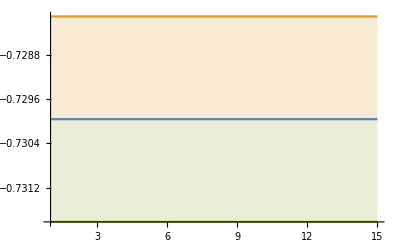

```mathematica
Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,15},Filling->{3->{1},2->{1}}]
```

```mathematica
SpoilHWFLOPlotN3=Show[Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,Length[meanErr2[[5]]]},Filling->{3->{1},2->{1}},PlotRange->{-1,0}],ListPlot[{Table[{τSteps[[1,i]],meanErr2[[1,i]]},{i,1,Length[meanErr2[[1]]]}],Table[{τSteps[[2,i]],meanErr2[[2,i]]},{i,1,Length[meanErr2[[2]]]}],Table[{τSteps[[3,i]],meanErr2[[3,i]]},{i,1,Length[meanErr2[[3]]]}],Table[{τSteps[[4,i]],meanErr2[[4,i]]},{i,1,Length[meanErr2[[4]]]}],Table[{τSteps[[5,i]],meanErr2[[5,i]]},{i,1,Length[meanErr2[[5]]]}]},PlotRange->{-.03,-0.005},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]],markerlist[[4]],markerlist[[5]]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]},PlotStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau_{\\text{steps}}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3(\\text{NNLO})",Magnification->1.2]]
```

-Graphics-

#### QCD LO - gauss

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={430,430,430,430,430};
NWalkers=200;
Nf4α1LoopBig={0.4,0.4,0.4,0.4,0.4};
aList={1,2,3,4,5};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
csvData=Table[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"],{xx,1,Length[aList]}]
```

({mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.08317293080559243, -0.08522320443921047, -0.08803377339802948, -0.09126407018555502, -0.08218849733671749, -0.08034529435530509, -0.08155865663869401, -0.08100491152022718, -0.07907260062507734, -0.07936625527075113, -0.07983370574764015, -0.07340730808464668, -0.07158686874368453, -0.07955849334174538, -0.0733181690415159, -0.07550195478132375, -0.07926480236248593, -0.08087051579660745, -0.071271471254871, -0.07361679221750249, -0.07408460174197104, -0.07704896255842243, -0.07671341824890668, -0.07214774423841454, -0.07340011228033515, -0.07426079547747702, -0.07325799788138888, -0.07784475805403296, -0.07578248833053812, -0.07756822568686966, -0.0775391293909645, -0.07363967260876086, -0.07579176518309372, -0.07718354275495648, -0.07236358048544134, -0.0693141062425492, -0.06737042769341611, -0.06734486919092442, -0.06719820980093076, -0.06968846131544008, -0.07060545684193259, -0.07492857222619773, -0.07893377627999046, -0.0769248172641834, -0.07594168527734274, -0.07292830784251458, -0.06904538966233703, -0.07164651792819754, -0.07773311237294671, -0.07076193897765946, -0.0719607620226699, -0.06863071850378932, -0.0747229094567454, -0.0677183119699023, -0.07037123254488489, -0.06927161793825415, -0.07009172892019143, -0.06900324830918826, -0.07196188803723715, -0.06940077139811697, -0.07030725340412884, -0.06973673086863304, -0.0733248297478574, -0.07563142935733701, -0.07191518427778526, -0.07322834047624935, -0.0752566700026122, -0.07373422449378997, -0.07472300705043122, -0.06847191286273994, -0.0676315169291707, -0.06950010978454546, -0.07013106403970207, -0.07720509079845397, -0.07581195623728808, -0.0706423768696846, -0.06945335972300316, -0.07182880341529224, -0.07596296371698404, -0.07516110685572894, -0.08115445863851341, -0.08116661263182937, -0.08579897632862071, -0.08843913463830402, -0.08704679352148341, -0.07772536424428658, -0.08240761965921763, -0.08306378600329754, -0.07985458160635829, -0.07546293365182341, -0.06970796425709146, -0.0672803536082342, -0.07514350710390591, -0.07973191697619869, -0.07269066332151328, -0.07539548194974381, -0.07614782447465403, -0.07484423052324028, -0.07163432982154617, -0.07351578475777673, -0.0800900619094147, -0.07705767608717472, -0.07839114855344043, -0.07443820698872428, -0.0876086088987424, -0.07918567014142877, -0.08310593174819347, -0.09467178268484552, -0.08224580014119783, -0.08304141546714273, -0.09149210056979262, -0.1438363602249588, -0.08396186858481673, -0.08320769905491392, -0.08308654163779998, -0.08426346480234097, -0.10250947350359378, -0.09154937914294561, -0.09462501720676103, -0.09104151458675303, -0.09617103946608828, -0.07807224095730037, -0.07445512946198683, -0.08332923582529576, -0.07531253661461422, -0.07567829101187959, -0.07423014969272634, -0.0708152673243676, -0.07145309911513445, -0.07130684649525774, -0.07540535469145458, -0.0768057767081573, -0.07678630465484622, -0.08040018445386883, -0.07828860043762387, -0.0785358439964506, -0.07518245501395363, -0.07255075450308483, -0.07637778851701522, -0.07875216127170695, -0.0810814892907784, -0.07628254632142473, -0.07350177362482639, -0.07308690529893688, -0.07369654480120912, -0.07562962120889569, -0.07543049985442161, -0.07144843772599714, -0.07016720150454557, -0.06789412530885956, -0.07043878776599091, -0.07107692322166373, -0.07088659385983957, -0.07065009945267968, -0.07069522960059114, -0.07207826516639851, -0.07358058298979546, -0.07745744273465838, -0.07778962755375533, -0.08235722079170944, -0.07987822947511733, -0.07875435822322407, -0.08118791817534815, -0.07756357997893565, -0.07528625730014073, -0.07790772622037528, -0.07562800330620631, -0.07565548663605587, -0.07211584260824766, -0.076267415777724, -0.07785725477505422, -0.07686408816482815, -0.07177368807710738, -0.07207999272635357, -0.06593828928050074, -0.06491233691454504, -0.06890688574891403, -0.06919803519890055, -0.06924995652476504, -0.0687942569509365, -0.06711692525487191, -0.06845771098961609, -0.07136442885952703, -0.07327964360705748, -0.0788160762761346, -0.08104422841678004, -0.09136901776167798, -0.0878571124795005, -0.08373249512437969, -0.08334797596659065, -0.08478494848127714, -0.07938557085410164, -0.0743949211574229, -0.07163577063848632, -0.07833782099385693, -0.07608496876567085, -0.07987728451321784, -0.07794692351158956, -0.07949520685818931, -0.07486269966332369, -0.07477141989396444, -0.07223837846520226, -0.06908061948547592, -0.06582458719576931, -0.06460379216883788, -0.06477323121228436, -0.06820373576808643, -0.06634818575562743, -0.06490211413219811, -0.06315589654418721, -0.06331931387315512, -0.06302116426947586, -0.0651862639918502, -0.0690787527212882, -0.07286172897511492, -0.07238346502025195, -0.07653345877032011, -0.07444422810209403, -0.08497218472829486, -0.08206122309393983, -0.07961086898074861, -0.07452437680569661, -0.06671652444692905, -0.06116312067897193, -0.06145486442441291, -0.06589888535957279, -0.06241556788680184, -0.06313764817656636, -0.06347718761309624, -0.062286085268880215, -0.05993907458779149, -0.06458193827854201, -0.06114210074236843, -0.060728269111659995, -0.06341193932057022, -0.05967998600219109, -0.05726435430942825, -0.05960930537013908, -0.06350490499521355, -0.06919955423448154, -0.06788934933734193, -0.07327359439302761, -0.06684341994370457, -0.06616098801916039, -0.06428440826035478, -0.06047975207188376, -0.058853499415736504, -0.06162532022430422, -0.0627103495097785, -0.06713047365772705, -0.06519352880469119, -0.06791302151014984, -0.0648594775010656, -0.06376223929642322, -0.06399562191766275, -0.06128749726781821, -0.06453089945851455, -0.06741392513128412, -0.0602485785905035, -0.05760065175465156, -0.0592686429072075, -0.061822357049712805, -0.06165576039244273, -0.06341250275121857, -0.06241438467476185, -0.0634222479508585, -0.06341435566470456, -0.062194451718275895, -0.06571127309479283, -0.06534928723158448, -0.06680130746602334, -0.06811006573433716, -0.06691789319975026, -0.06655924102368228, -0.06798263356593921, -0.07115664613558426, -0.06857396218419684, -0.07356606339438425, -0.07774163603502252, -0.07520581053621846, -0.06915349305742252, -0.0642802594921163, -0.06555214619079719, -0.06832029375426373, -0.07177657663094049, -0.10078074721766865, -0.06936135298684691, -0.06817517334970917, -0.07517755549301951, -0.07107371925471932, -0.06701223755442763, -0.06737527973552992, -0.06404443374267067, -0.05915668883318465, -0.06139262931025735, -0.060193435955445546, -0.06016044955268197, -0.06538232471497041, -0.06307507061947827, -0.0668202024562081, -0.06613525558968296, -0.06645367531174096, -0.06623847783945298, -0.06813800199622125, -0.07171344889338727, -0.08108227290760989, -0.07022439582524015, -0.07005335619586434, -0.07527407274291978, -0.07256235189404918, -0.06897173466003424, -0.06904663617275096, -0.06785966761523893, -0.07701545188515665, -0.07212556462870044, -0.09369995406913253, -0.07461781041377062, -0.07742468986884352, -0.08875269588722814, -0.0740130983323804, -0.07269105877302502, -0.0704597038969695, -0.06969259787410491, -0.06962620643993893, -0.07207136261605239, -0.0747082908766795, -0.07292414914504071, -0.07317375596703435, -0.07629677832518557, -0.068573197522587, -0.07061762783776136, -0.07085265320893457, -0.08040053797961276, -0.07049858722654564, -0.07099608279780488, -0.07190982462078559, -0.0728485403429706, -0.07106686028084261, -0.07508334882379154, -0.07437314574366884, -0.07715259608052515, -0.07150417517081585, -0.07161709088481014, -0.077100396264855, -0.07311731165917612, -0.0809042990863596, -0.08256656682548799, -0.077830590822796, -0.0817946548557141, -0.0959858652455789, -0.07752522964373422, -0.0686249353559864, -0.06895149442467179, -0.07249596535471486, -0.0739154160919212, -0.07769683496607248, -0.0718831335188453, -0.07653271658680877, -0.07146388241681077, -0.06941067716069658, -0.07287937409860748, -0.07539777099863888, -0.07170198854219245, -0.07842834945636053, -0.07509123186620505, -0.08668220939802739, -0.08205244305718608, -0.08465327411878201, -0.08917865514311145, -0.08439954148273247, -0.08822745774703844, -0.08281835862053233, -0.08416268125116688, -0.0889603646378271, -0.09455068425323533, -0.08965171180527773, -0.09831464669989391, -0.08966181197756097, -0.09135054573919166, -0.10053398838280933, -0.09790448592366295, -0.09734377404330324, -0.09739122029784465, -0.0939410174374102, -0.08630270342401809, -0.0873426677404468, -0.08528824927565756],[0.007731875728108595, 0.007803137337419653, 0.008651136175079724, 0.010515329458077576, 0.006401642307882755, 0.007120595393555722, 0.006503614295598716, 0.005763202468018763, 0.005200487981765413, 0.005305406882485705, 0.0054350909630653315, 0.004387098030798998, 0.004350710658098453, 0.009402535661049113, 0.0055200303796379465, 0.0058798976744395305, 0.00564710842275489, 0.009228076078502389, 0.00388364739771787, 0.004341917877291521, 0.004354380088090873, 0.004579838640020334, 0.004893261423814566, 0.0036725102673583155, 0.004299619024065652, 0.0043783095698713605, 0.004230031743222302, 0.005388773186553543, 0.004862252457491845, 0.005665971426734705, 0.005667595875578398, 0.004988576710980388, 0.005764055393701972, 0.008166571953884648, 0.0051495523669745896, 0.0038205923875233652, 0.0035523489679310945, 0.003777326470349063, 0.0035305094593168773, 0.003834850304495923, 0.0042138151747693935, 0.006437742610207817, 0.006776887346231589, 0.006885026904167995, 0.005525438320950225, 0.004730600963307471, 0.0030845009205141853, 0.004718438851697824, 0.00839090705348679, 0.004873277093260536, 0.005134703676055595, 0.004707740105547018, 0.007998037865587311, 0.005782606409977946, 0.00526885565830232, 0.0050594801225208996, 0.005647669915791357, 0.004535446278516215, 0.006479977586453724, 0.003987737898359008, 0.004160073327738783, 0.003243679135809058, 0.003927635913355937, 0.0044682856287252435, 0.004212971785286837, 0.004476871491826341, 0.006048734949895488, 0.005104147780729468, 0.006037087470899348, 0.0036694596822546563, 0.0035627812018185524, 0.004812251882912398, 0.004743807080339347, 0.007752472732950686, 0.006909858399848679, 0.005262123484344076, 0.004650977721008926, 0.005728099358905406, 0.009670237544934146, 0.0066334962829430804, 0.009561236815917666, 0.013003675797430827, 0.010113056705729172, 0.01311401806287729, 0.011516455858392078, 0.0053483221674262066, 0.00625828777359154, 0.0061128024904927745, 0.0069257956218757195, 0.0059617094849027975, 0.004854145003159047, 0.004259630437240326, 0.009824108588597521, 0.010683175147380843, 0.00523454962356175, 0.006342391962882097, 0.00733983081610045, 0.006867891699263854, 0.006537360332767931, 0.00691544241657276, 0.013604990440894556, 0.011533903043389382, 0.011929092534489996, 0.009782116627055908, 0.02202858339354143, 0.013720798203746394, 0.014429740650916319, 0.024308550800521866, 0.014117712276210607, 0.014013181443974242, 0.02132897482402131, 0.06722946135084364, 0.011528218851607172, 0.00830882558422746, 0.008699724005692312, 0.008159853039541377, 0.019144637890485764, 0.015789936989422985, 0.018590131717436, 0.014808009129652718, 0.01503547660531441, 0.007112705228279519, 0.005545052045226082, 0.009235663730602462, 0.005680794307509119, 0.006832132441167686, 0.007128479896298207, 0.005544024559359642, 0.005226549890791012, 0.006395938218806744, 0.006881349583219039, 0.006826207364537835, 0.0052081887057669725, 0.006243641220462326, 0.006045309844951074, 0.006387841668052398, 0.005775761644734747, 0.0075233106568841955, 0.007364890177304091, 0.007230540567689769, 0.005881670230574095, 0.005810072213528914, 0.007352306031337954, 0.006872888680294186, 0.007801313923787049, 0.007816231168765661, 0.008380768463848021, 0.0058448476230274805, 0.005265142545273794, 0.005143789209392172, 0.0054134272353967595, 0.00572596205217456, 0.004478879381478542, 0.004614009269854606, 0.00449732442184183, 0.004598531744213617, 0.005307330750371194, 0.007074565813827547, 0.0074356336920934525, 0.007989863878805199, 0.007005147441100704, 0.006238093473145731, 0.00683737476501941, 0.005569895157618421, 0.005130195371700951, 0.006239966888571378, 0.005946780227023397, 0.006341271970355741, 0.00643872605663621, 0.008163972343875977, 0.00912969029019606, 0.008577295303639258, 0.006691300691732724, 0.00853783713956356, 0.005828070858575067, 0.005156909189028864, 0.005182994766125776, 0.003949829609549541, 0.004221681606203793, 0.0061577940863832715, 0.004141786021352693, 0.0032971228246504677, 0.004088978713375934, 0.004540120841849861, 0.006684023911510881, 0.008170607403652358, 0.01013510908420868, 0.009895288248639757, 0.009175613337479547, 0.01034998681274208, 0.010544798426423663, 0.010512585453774793, 0.009596032780152298, 0.007754885675469738, 0.010370802498256107, 0.009761938087278522, 0.010587862226510883, 0.009230616086477794, 0.007859719228222092, 0.006765890098060396, 0.006779948581237523, 0.006767062985222158, 0.006145205383547412, 0.005748108906172589, 0.004780529993540566, 0.0038412476430205785, 0.004775091616893677, 0.004847536088620594, 0.006202326646378272, 0.004993239910991603, 0.005118813907453228, 0.0047159082598324815, 0.004948978006357225, 0.006310232664673688, 0.006945357394295404, 0.006315900601958244, 0.009048335792597945, 0.00864549545581718, 0.015187312324805044, 0.011278938465960077, 0.011246001922421736, 0.00838869850064246, 0.0046429439825667876, 0.003128492589937798, 0.0037185209327514615, 0.005494887620470153, 0.004600444013108546, 0.0033756539854896575, 0.0029140856496329866, 0.003031971523096031, 0.004460416512780585, 0.006570190342144728, 0.0037275854208963827, 0.003943178749274444, 0.006937371452746751, 0.005806307809433364, 0.004239038201325574, 0.004746820501196056, 0.005535056046327754, 0.007961355390883346, 0.00681583781096868, 0.009361272664833793, 0.005078508924665067, 0.006042237555310619, 0.0064042362563972695, 0.004338994135779965, 0.0035814084456655547, 0.003715199725194812, 0.0050583231527823545, 0.0064008850260841845, 0.004750205302748716, 0.005519411858318849, 0.0034728354888858655, 0.0033813717696127648, 0.0048653168306808225, 0.004419788940162707, 0.008081969206711236, 0.011770124578527013, 0.0063541159596677025, 0.0036179655873258346, 0.005129394144724984, 0.00440569724577591, 0.004689430554263853, 0.005624202002179297, 0.0032123983203737397, 0.00436222754645726, 0.0051058464224956, 0.0052820613150244364, 0.007026934043482754, 0.005511130397093516, 0.005920666804145339, 0.006220853077325059, 0.005742813050769551, 0.005265843589285298, 0.005431208862187867, 0.007339352899974062, 0.006944717576853848, 0.01062861843613176, 0.012922022868204862, 0.012323485901039703, 0.00640533811089913, 0.004250875667692723, 0.004916718077580719, 0.005593627059569754, 0.007092012256718926, 0.02875019513146378, 0.0058328973550090205, 0.005570680922103561, 0.009253258043172272, 0.00710628160902256, 0.005925221108196309, 0.004996563471758347, 0.004659774640057241, 0.004372007718541642, 0.004692863420907368, 0.0050350253718511925, 0.004947877835454674, 0.005458120969819476, 0.005242663761805441, 0.005301183049810511, 0.005717119630970136, 0.005420221947781901, 0.006533076823667863, 0.0059163307409061, 0.005337277592693614, 0.01009364306879027, 0.005685487865611885, 0.005588401254363974, 0.007294607964658053, 0.005770720331803915, 0.005222670709945429, 0.00523868591333424, 0.004903712696061495, 0.011250807460082267, 0.006398657366072629, 0.024389021877099324, 0.005681726307320549, 0.0063504341100353474, 0.014304532242200631, 0.006145959822779941, 0.0068514889905520624, 0.0073506467483890415, 0.006960435261845338, 0.005879618237661344, 0.00604639481432382, 0.0072825789689671, 0.0065237172944804765, 0.006732808360550754, 0.008058707894231208, 0.005228651408624577, 0.005835459014611818, 0.006757531660874266, 0.01233606426927784, 0.00674838159987576, 0.006362110806369467, 0.006835625759276874, 0.005677911550230025, 0.004784670988143327, 0.005054535124136257, 0.005089248113560895, 0.007789870994456721, 0.004620936486117593, 0.005880842744262647, 0.006953615793358939, 0.00514259651547997, 0.012526949916443974, 0.012807784609426854, 0.00898139236002786, 0.013470632773669593, 0.024000683154670892, 0.00980395486698093, 0.005144842626388109, 0.005327315295347996, 0.007727817055329156, 0.007402419530963612, 0.007363500883707075, 0.006005906895497378, 0.00956764556368986, 0.006040266249320782, 0.005400493232896099, 0.00686789193867347, 0.00726376823874215, 0.006263461801228932, 0.009500437653819938, 0.006183807730248221, 0.011187842556432478, 0.007448252295001812, 0.007638745325329554, 0.010486130707124564, 0.008801814290939864, 0.012040042679326093, 0.010503177282850093, 0.010098848083061406, 0.010456221730056248, 0.009864352244847083, 0.010253317650101582, 0.010906109511073177, 0.010721581607158916, 0.008765400623124121, 0.014884286691284394, 0.013273093957733541, 0.016148411838729244, 0.01491674691773665, 0.013939014189492551, 0.012544699427967263, 0.01295296065136152, 0.011790210350252371],-0.0670047,0.000499792,0.72931}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.05679420278359956, -0.05628143524045573, -0.055727226712236545, -0.05742089924636391, -0.057994996852864564, -0.0570298184340412, -0.058364333216633424, -0.05818156403416854, -0.05721113908941561, -0.05664603386130768, -0.056589976265671124, -0.05682150397740917, -0.056320756022741475, -0.05669179362996117, -0.05673980419197343, -0.05821625293797116, -0.0565289593421034, -0.05666380987934673, -0.05693094633667413, -0.059043765316208356, -0.05844875718511056, -0.06098780296446903, -0.0587349745358216, -0.0586700970011926, -0.057988246059912395, -0.05982906730537334, -0.06075923361927219, -0.05977500510084184, -0.060883630706153685, -0.06316819581566872, -0.06111517228855569, -0.06160156729128211, -0.0604127941654393, -0.06333363422849773, -0.06070051967900462, -0.06166561331367231, -0.06173695089876878, -0.06213418238827499, -0.061454166551630454, -0.05833330779789316, -0.05586772331880276, -0.05480947932431003, -0.056509745390793446, -0.05496882426836389, -0.05625544906400561, -0.056156758483831705, -0.05567359784986231, -0.055278942996216364, -0.05339284571052681, -0.0536989877367707, -0.053888097070529536, -0.054148403625534865, -0.052286631675686555, -0.05322012085942222, -0.05402451701429166, -0.0528714082217228, -0.05278166829042534, -0.05290965379079659, -0.0531422056425047, -0.0535343637774473, -0.05279612464568908, -0.05310563915340779, -0.054444743526478684, -0.054613853943781716, -0.055355542840108685, -0.05434964608887025, -0.054306185928664485, -0.054062868255933406, -0.05551603729401614, -0.055529224025692506, -0.055300018759850245, -0.05503880453301539, -0.054247623246112577, -0.05515600540725125, -0.05434440987773936, -0.05465616463308336, -0.05399869482941156, -0.05495289887824661, -0.05447966847135237, -0.05475076508551658, -0.05413002740486419, -0.05460790380489165, -0.05469756683197892, -0.054660577594251414, -0.057517163291732044, -0.0566134965077424, -0.05682089685715457, -0.05695556643896689, -0.05738684164078439, -0.05609684119826738, -0.05748145997003533, -0.05728837992772875, -0.05759251997101901, -0.057530625387116945, -0.05893584242205067, -0.058586265497326075, -0.05710329920383031, -0.057012999006940665, -0.05721699080988507, -0.05820604713870744, -0.05583618129863497, -0.05707046624793201, -0.05764239136319187, -0.05781413574595361, -0.05746864640764527, -0.058247107396274894, -0.058418253202946094, -0.059013505292283955, -0.05781759152679891, -0.05895311382939186, -0.058565932866792896, -0.05945900774690413, -0.05881173515268248, -0.059425326257957566, -0.06336587039630676, -0.06324819281338567, -0.06345088367874538, -0.059995753943193175, -0.06721503072451449, -0.0616775852909171, -0.06478255833357936, -0.06261188806445525, -0.06039802656086352, -0.05908895759232899, -0.059965869383423985, -0.06079430099727674, -0.06246475132910136, -0.08816693193477461, -0.06875335176601645, -0.07445215367714572, -0.06573564796505647, -0.0683744384068331, -0.0755275168474075, -0.07257956471551089, -0.07722599453547598, -0.1234277119690223, -0.08675742360948908, -0.07357923338438234, -0.06889249568641752, -0.06734526973492751, -0.06737364785512819, -0.0695557825217955, -0.0627062100999491, -0.06340893458519847, -0.06319123447794024, -0.06452425083925925, -0.06240497402517582, -0.060474740867985766, -0.06067350849669358, -0.06006702831750647, -0.05933326562660458, -0.06033630214993029, -0.06125504532922197, -0.06041466526888087, -0.06062751980992937, -0.06072686368678606, -0.06304781108196364, -0.0655667491258714, -0.0639481238833832, -0.06578789183949234, -0.06847283472355901, -0.0675387474743481, -0.07087726892625013, -0.06851933661953528, -0.06822529906368013, -0.06748623884377222, -0.06674418424146772, -0.06468698039839299, -0.06591079524296903, -0.07012973468245813, -0.07040264638259765, -0.072693219294918, -0.07405184648325407, -0.07155884422321494, -0.06642224342867806, -0.06779019870139663, -0.06700742844394818, -0.0704384477682166, -0.07446305562874257, -0.06901660944866717, -0.06882507344885525, -0.06750507083804845, -0.06810468349543145, -0.07635282806264357, -0.08149343434982333, -0.07467240363821807, -0.07219037663670182, -0.06928095450702434, -0.06897166461841239, -0.06853735079095495, -0.06951740966825594, -0.06987589198248913, -0.07171046301656302, -0.0671875785183769, -0.06972891231113555, -0.07071544092743534, -0.07018970386156126, -0.07589277235296447, -0.07014501404840144, -0.07504132354634618, -0.06671276463626995, -0.0685279780246045, -0.06635945401201268, -0.06935711805670282, -0.06712385827811522, -0.07095495769701554, -0.06516215900991308, -0.06607129573725322, -0.06561666136024005, -0.06570890458968234, -0.06451678183307584, -0.06435776119137586, -0.06950080162864263, -0.06864665532856887, -0.07045021278921494, -0.07568329391367344, -0.08241542635864324, -0.07333526652469663, -0.069888744224587, -0.06741807542368879, -0.06960488501120791, -0.06853434977554304, -0.06799160679298671, -0.06596041664891904, -0.0664804403971847, -0.06540834223856784, -0.0662358949713954, -0.06667781389268213, -0.06469572269682415, -0.06560825695825426, -0.06400886571512557, -0.06255612197290764, -0.06467099182722597, -0.05941642764767298, -0.058742551610107885, -0.05851342679440166, -0.0580422471448774, -0.0589063862423869, -0.059772110688919425, -0.05904576891020129, -0.05969982601977702, -0.06091126739801727, -0.06173283065989177, -0.06495585335845289, -0.06334228054763098, -0.06651639383215655, -0.06458487949343211, -0.06347118083449055, -0.06219295278082835, -0.06281888176186705, -0.06144412620235534, -0.05848981593071072, -0.05972341770105092, -0.05896643658518905, -0.05925696021551268, -0.05936252891585412, -0.05928227790254652, -0.06214721177168705, -0.060218300438323415, -0.05919673573870877, -0.05786638522065441, -0.05675090735502836, -0.05660602697470159, -0.05657011991604927, -0.0575165011356723, -0.05868682765771399, -0.05902234251113754, -0.057537734606219734, -0.05868006994797472, -0.06083362659110006, -0.06146905060237611, -0.058836950565639125, -0.059771857795323784, -0.05569275535688684, -0.05600325152254068, -0.05610853061976727, -0.05554968492448367, -0.0579541716086206, -0.05567121404301847, -0.05574045355447863, -0.05676311247464322, -0.05534322534169101, -0.054824739702476456, -0.055399122535290155, -0.056354161777282634, -0.05734671591454556, -0.05932588923321308, -0.062440541109672204, -0.06653449330497488, -0.06251830404394988, -0.061567800586503796, -0.060501705526426405, -0.05994992951806111, -0.05868436477786691, -0.05791591736389746, -0.05935954877469685, -0.058881307171560544, -0.05903687246879613, -0.059695021983285204, -0.0652756852725442, -0.06211230484907887, -0.060181235456128745, -0.05843647895954247, -0.06224273447971295, -0.05932030210792904, -0.05916765594769493, -0.06011478995550151, -0.0628563995581356, -0.06450129225948219, -0.06672281996354834, -0.06492085374013161, -0.06734845676737243, -0.06623499927237299, -0.06645285375012021, -0.06594499730805366, -0.060756329772013666, -0.06024737892900453, -0.060637654674420685, -0.06075614904035049, -0.060664222826725865, -0.0603858560813393, -0.05846474565727263, -0.05852795225600325, -0.05791387547238855, -0.05797193918414256, -0.057494213892733174, -0.058677127175861724, -0.059672181591648984, -0.05975953034185625, -0.05838349682809044, -0.05943734121075152, -0.05843677315703507, -0.05946983109665775, -0.05988163065255877, -0.05907961855388541, -0.05947609072756876, -0.059207710914241395, -0.05860994829132806, -0.05995825294158934, -0.06066968011659244, -0.06135062532251972, -0.059620497375302416, -0.06063936485545029, -0.06286948954206535, -0.063418926177373, -0.06442264930856756, -0.06256270084929902, -0.06360383843353426, -0.06670972068594631, -0.06322629572415756, -0.0631485619437993, -0.06254004400060577, -0.06329860981963065, -0.06432023935321889, -0.06340287281898906, -0.06427812691362764, -0.06573973852640327, -0.06580711774157953, -0.0662133644978205, -0.06577515833394937, -0.06512595150517346, -0.06476622189957174, -0.06638517008937644, -0.06767630295477531, -0.06675792062526742, -0.0648647362234447, -0.06327934602957713, -0.06733181030267674, -0.0679363549310428, -0.06777009701499817, -0.07087773212163809, -0.07251439012624653, -0.07386976980630623, -0.07239807588888231, -0.0665647405495887, -0.06854134662865626, -0.06753411262318869, -0.06572435403738808, -0.06812182025184721, -0.0674409579951708, -0.06351866345274765, -0.06323319128594453, -0.06453945761869996, -0.0662953397813885, -0.06762052168871156, -0.06343564703282127, -0.061598815481841575],[0.0027334436541052256, 0.002222498959210659, 0.002109881250027786, 0.0025068658730571197, 0.003028511506947146, 0.002821256648866156, 0.0030495306259718533, 0.002682756592453154, 0.0024165757284089194, 0.00220891643891614, 0.0024086427607228206, 0.002661442720995226, 0.002341728685606383, 0.002209267756372236, 0.0023959798329199985, 0.00347426080136557, 0.0023005516971436432, 0.0023496390243959277, 0.002542372124845662, 0.00371406548938851, 0.0029942267546777365, 0.003978202430240957, 0.002643259175662567, 0.0025179121970125857, 0.002278039714349924, 0.002928038537538655, 0.0032592090992200674, 0.002835665119260847, 0.004221426109296903, 0.005789017431848425, 0.0034423454778035162, 0.004620036840803801, 0.004027851737385195, 0.0062199444230153335, 0.004224246777059007, 0.00469450729615358, 0.00475437815603027, 0.005894761875431035, 0.005451868532871147, 0.003394165231222862, 0.0023104906314365243, 0.0019265427337727297, 0.0027134650013167774, 0.001956251610274701, 0.002211118589140475, 0.0022163127177378863, 0.0020506167090370785, 0.0020111171657239365, 0.001591416407705694, 0.0017877826417373676, 0.0018005501350643021, 0.0018558783477915374, 0.0014899390490241088, 0.0018069542737826835, 0.0026950539326383535, 0.0019363200844331894, 0.0016169489026323764, 0.001570182409030936, 0.001711881689634558, 0.0016601936865675876, 0.0014754602198352288, 0.0015039322868171815, 0.00169020855374701, 0.0017944565652676324, 0.0019883040622314043, 0.0017723469496069319, 0.0018562271920695393, 0.0019229828886804772, 0.0025060824277509273, 0.002821623936748021, 0.002396291097244747, 0.002239220506527764, 0.0019153006259673873, 0.002124617036822943, 0.0020393441140026604, 0.002147510450044778, 0.001890894943554364, 0.0020832903536794796, 0.0019962775726917476, 0.002083076993655186, 0.0019781504701591743, 0.002199301017483649, 0.0027054482781722453, 0.002403953376767892, 0.0036877772877589483, 0.0030330823932422325, 0.0032677365733706494, 0.003179647596606752, 0.0037201644544644454, 0.002972597794469481, 0.003249875897868712, 0.0029017428955423687, 0.002852981739370375, 0.003007028232057514, 0.0036125397939044063, 0.003168013643182065, 0.002752894690882385, 0.0026954640938725996, 0.0029043554087416377, 0.0030267718521317204, 0.0026428791182512524, 0.002890788472119144, 0.0031253889797964456, 0.0031927575377278077, 0.00315216944585005, 0.0033335436217431253, 0.0030907997975547267, 0.0032312417240115457, 0.003091611465229406, 0.003410229487249958, 0.003287429362335307, 0.0036716533234169004, 0.0031767550244674357, 0.0034270727611997666, 0.005730701772309732, 0.006187924069166166, 0.006051659429151854, 0.004665146936627964, 0.01091936635043927, 0.005400694579484116, 0.006726188918005645, 0.005013854542909651, 0.0037078485694586054, 0.0032168289261918386, 0.003409110052391688, 0.0038111261388995192, 0.006188926387158341, 0.02842863259175685, 0.01023114673888731, 0.015437248277334194, 0.00680558827877568, 0.00994121799942859, 0.016803302499679155, 0.013557683415328895, 0.0167005096069213, 0.059362667866142735, 0.024196245544386225, 0.013425900080126917, 0.008704740167766664, 0.00672846197367943, 0.005156857755186661, 0.006058785716534563, 0.002921964699670161, 0.0030882202988651206, 0.003724793938894714, 0.0038887774992489295, 0.0034927062126542912, 0.0029973327368776137, 0.0030353729813499338, 0.002915401703305494, 0.0028251190509552843, 0.0031685717067244613, 0.003109290318439773, 0.003140339654551497, 0.0030139557390878886, 0.0027991199901453634, 0.0036314336584122556, 0.004811006677443322, 0.00383343778577213, 0.004310196137473696, 0.00478900720274284, 0.004698481633231155, 0.006279845835048239, 0.004697226192540677, 0.004417481524434524, 0.004518506609545979, 0.004077016617519607, 0.0036599042075541434, 0.003899331623731527, 0.00465506693490273, 0.004806307128875976, 0.006536516585784605, 0.006845426344100386, 0.00539927185358652, 0.0036897578556199283, 0.004346038380629525, 0.0044270383913942776, 0.0062059853147618796, 0.00741351501383078, 0.004829189632772115, 0.004793976252729589, 0.004698525209486109, 0.005340589639781083, 0.009939198957795605, 0.011404275361177442, 0.0067180491440405905, 0.005616291021319347, 0.00471417978664747, 0.004571439235551906, 0.004402719372334383, 0.0063694932605461805, 0.006654464309161086, 0.006779331878065094, 0.005166402914606286, 0.006249899775788358, 0.007009622291649131, 0.007735546326289313, 0.011850681050660733, 0.008334924826964116, 0.012365627504798655, 0.006081441731073729, 0.006371774727158135, 0.005340574902610518, 0.006458069508289597, 0.005549698927842391, 0.007244750484439611, 0.005540628622245746, 0.006220192293990185, 0.005758383776730007, 0.005692038110037772, 0.005432898878978039, 0.005403263260025134, 0.007353150870740109, 0.0073283420203821125, 0.007855962480030548, 0.011566125737208997, 0.015250675121943153, 0.009870809754570277, 0.008433024531075032, 0.006301940036376651, 0.007205235090473726, 0.0065423928187915755, 0.005923868880406149, 0.005149216542701844, 0.005685701995322589, 0.00556162565974987, 0.005682908138451682, 0.0060361239120303774, 0.005405325374878958, 0.0056086993246162, 0.004897221423665509, 0.004300135217784563, 0.0053792281611001235, 0.0034819803352452816, 0.0033294845652010077, 0.003391745161004429, 0.0030700569541518845, 0.00333957955688551, 0.0035115062520049713, 0.0029092591181248935, 0.0032147770095111643, 0.0038194636620899605, 0.003939466502322935, 0.0060200470087886536, 0.0053682700018787095, 0.007644933019784836, 0.006157393444166829, 0.00512521977533088, 0.003995343728167854, 0.004674239051964493, 0.003920809745285118, 0.0026806185743153536, 0.003148615019327804, 0.002878234476363938, 0.002847946884060547, 0.002858282843945486, 0.0028436057138975833, 0.004250192007499461, 0.0033390737516296133, 0.0031195542137057975, 0.0031045595474125456, 0.002779528186626698, 0.0025361105918456175, 0.0024625801137075944, 0.0027271486738271148, 0.0033060308744151785, 0.003470835445811768, 0.0025998783687942355, 0.0031302975453680703, 0.003812093302719239, 0.003730273043039409, 0.0032700734073176046, 0.004309748377337241, 0.0027090621771286376, 0.002720734924120019, 0.0027752594491910775, 0.0029123037366541996, 0.004121740775502049, 0.0029665853179259394, 0.0027437620485755818, 0.0025845427634989303, 0.002155115640065576, 0.002113337558359383, 0.002681710114977835, 0.002969588035446291, 0.0033508968958700326, 0.004489168856151213, 0.006464416099851848, 0.009430484974002317, 0.0066333022607715725, 0.005193561179623639, 0.004486690679225425, 0.004618812395343549, 0.0040092438787839935, 0.003175349376227463, 0.003918949870260945, 0.003586184304128659, 0.004046499994089374, 0.005028989298260252, 0.0100650896457517, 0.006921673072704918, 0.0053084149627216715, 0.004605213454758915, 0.005793799948498619, 0.003980289070877221, 0.004060061171209625, 0.004121758105310994, 0.004842523190831178, 0.00476515515900066, 0.006339649205196157, 0.005351475535640386, 0.005499657162666144, 0.005454967553930139, 0.006386418553987852, 0.006899722251601052, 0.0038275270259804715, 0.003463839572854183, 0.003805255671443482, 0.003896669709417868, 0.004478605549122641, 0.004566900340715341, 0.0037993604293382, 0.003904001191832584, 0.003656804918264249, 0.0035006743490992804, 0.003231928027019506, 0.0034881710359911553, 0.0036340096929099535, 0.004130207640979969, 0.0029587151422251637, 0.0028695441741703335, 0.002175800341517815, 0.0021897671553223696, 0.002334307143391056, 0.0021711949238804665, 0.002447779959145715, 0.0024572567464155692, 0.002370231576533794, 0.0027122554764939877, 0.002797751687559613, 0.0029790979514659754, 0.00254690568506099, 0.0028678023737034627, 0.003283354324667364, 0.0036033680263243524, 0.004226330972516165, 0.0033353697699839892, 0.004456687134880804, 0.005910716219160604, 0.003927977211645785, 0.003962835343124958, 0.0036668261484341996, 0.0037164097636731386, 0.004078330982857719, 0.003276051284160749, 0.00413278309763006, 0.004307570846381998, 0.004377957048095574, 0.0050957763875355624, 0.004509147477660704, 0.004447433636991909, 0.0038727604549755688, 0.004976109741144025, 0.005267403893892263, 0.004806661641532813, 0.003963532554270677, 0.00375985898445838, 0.005034466348049474, 0.005346890154370108, 0.0055507659030021835, 0.0064482016912077115, 0.00847180133122492, 0.008855633701569061, 0.0071298290171507555, 0.00419323629084868, 0.005775403212377425, 0.006712560219930805, 0.005138233119158495, 0.006309811787849261, 0.006218064287844379, 0.003678535853085068, 0.0034473990038397535, 0.0044165736942525565, 0.005645466385976412, 0.006598960135296161, 0.003941536353448772, 0.003090690103788009],-0.0543209,0.000502515,0.630393}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.04688127024056521, -0.046792229454234426, -0.046188577080070375, -0.0460329085163349, -0.04613202002512266, -0.04590501116562652, -0.04614078024427328, -0.04528441437550089, -0.045903628545610205, -0.045890276699613215, -0.045942082740179545, -0.04614431608372429, -0.045160981529956366, -0.044975611410273224, -0.04516934323851807, -0.0449854883931775, -0.04464456331224215, -0.04530205908222286, -0.04547410003107688, -0.045472176909392654, -0.04516873187873051, -0.04556693780129346, -0.04599573833418913, -0.0467479668383008, -0.04646524141197343, -0.04610619728170038, -0.04588461699142091, -0.04488245228375984, -0.04615463110957186, -0.04631594341804366, -0.04519953804721571, -0.0451115089792653, -0.044962133758772255, -0.046475840966305665, -0.045221404040210814, -0.04616645392824159, -0.04650366994219561, -0.04598592923585782, -0.046664845975102065, -0.04609735049199465, -0.0447459515157224, -0.045455362105706575, -0.04599027888879108, -0.04693665590125276, -0.045338743054229566, -0.04632287421842997, -0.0455029162256765, -0.04617574844222935, -0.04689658341248299, -0.047427862769675866, -0.04770967476731079, -0.04664172778830962, -0.04622684061760521, -0.04544434412847004, -0.04443908141272759, -0.04438983539740385, -0.04446065180663762, -0.04387013645274491, -0.04425537870634951, -0.04439214492173386, -0.0443848691688788, -0.04495007938140725, -0.04496843103207842, -0.04494719000453286, -0.04511017077391457, -0.04425387023689935, -0.04452464511709829, -0.044716021857532304, -0.04500309058989149, -0.04503693494067497, -0.04550560547028656, -0.04586848769717593, -0.04637101012398223, -0.04786343415918788, -0.04526139100892517, -0.04674325379725643, -0.045784280874761434, -0.045906458516454, -0.04574706225972619, -0.04643313890493099, -0.04581451743933403, -0.04562808018927166, -0.04527820181681895, -0.04509575623623893, -0.04507430518563969, -0.0452971441460384, -0.04549042846766454, -0.04566762684161142, -0.045003165171953456, -0.04554793084672131, -0.04564509906665316, -0.04634968292120042, -0.04638928395871405, -0.04643927533541574, -0.04648253464129993, -0.04666202582989281, -0.047125255628668046, -0.04750447603382396, -0.045898852554762275, -0.04778189507149842, -0.04904350147660445, -0.051399288677833194, -0.04897896103996905, -0.05252074007348297, -0.048638746719778726, -0.04973534103089716, -0.04717274506372452, -0.04716354057027078, -0.046494793586453004, -0.045803681163723006, -0.04482318825772825, -0.04456348363224869, -0.0445934868145867, -0.04439897851755482, -0.04442388424631571, -0.04408413711211423, -0.04419609624120736, -0.043683175472835664, -0.04366631576885033, -0.043650893181909324, -0.04404359998655615, -0.04330601546055891, -0.04389037734984517, -0.04328852853977613, -0.04329416875884162, -0.04319766681836909, -0.04357609220283471, -0.044488397860590265, -0.04443330243168011, -0.045017880313518305, -0.044124380682021534, -0.04407193834740194, -0.04427614626855491, -0.04369999003217764, -0.0438676852261336, -0.043210447051656574, -0.04340637511770075, -0.04294627576426187, -0.04265178048973276, -0.043507762203003154, -0.04387273815278977, -0.04353706626565256, -0.04378622408602015, -0.0434091643841397, -0.042940843927767376, -0.04281442356600288, -0.042234548225440906, -0.04193557460970671, -0.04176440188963714, -0.0421623224484949, -0.04194882809736692, -0.041848271339345676, -0.041872379730926904, -0.041932249991219035, -0.04195345028724387, -0.04166860839496889, -0.042289395743498805, -0.042846229219288406, -0.042744476621096504, -0.043386909807687356, -0.04329301066646366, -0.04339902427371133, -0.04314124657878993, -0.043560743051536614, -0.044135869801626454, -0.044157740907208934, -0.044330816324077746, -0.045115305545908396, -0.0466297946602772, -0.04819319870065847, -0.05363771485188625, -0.050473840298859214, -0.04757371084468351, -0.04968298516343464, -0.04730062700968154, -0.045772998246877514, -0.0450926125103021, -0.043891994600196466, -0.04499358038116548, -0.04525479139202792, -0.04608749997674852, -0.04448496829075127, -0.04462576328320587, -0.04597480574356467, -0.04487056285413213, -0.04596243538968714, -0.04558073462911936, -0.04577642733023518, -0.04536536856433186, -0.04505328012116483, -0.04598417617041038, -0.045538537119019014, -0.04626071264331786, -0.0459287155865234, -0.04681574818451004, -0.045684602028781884, -0.04629812428857974, -0.04693124629681258, -0.04777422176361356, -0.047017631102491034, -0.046438740700180774, -0.04679833072912136, -0.04473739657884152, -0.04371862291954041, -0.04457129834259773, -0.043698159591215056, -0.04351918002839337, -0.043303275325377324, -0.04334972755366493, -0.04321845226165648, -0.04351164532064789, -0.04384756846188984, -0.04359425142189344, -0.04444831613861513, -0.04483455786551649, -0.04544687826014329, -0.05009258597877221, -0.04629122324468461, -0.046948710961839016, -0.049062868256367236, -0.048701713155603225, -0.04705628912777714, -0.04684388626702796, -0.047430713113259235, -0.04869790651046915, -0.04785023038486898, -0.05635523779143413, -0.0637599477344886, -0.05035238264243471, -0.05138045945486618, -0.04902426467482942, -0.04972032385897499, -0.05182612512660178, -0.05054052015599576, -0.05042773574246967, -0.05010563733911802, -0.054672891843670884, -0.048521219472251007, -0.04791899355595884, -0.047309996741190546, -0.04710871820503811, -0.04816490975464886, -0.04768936109494661, -0.04721116317269194, -0.04683618276762613, -0.04661645442595981, -0.04640851244337913, -0.046322344896546616, -0.04655018439938715, -0.04711595709398472, -0.04682065691318433, -0.04687017462493346, -0.04745074286553217, -0.047230479779314355, -0.04739222912987312, -0.04748519409345451, -0.047090261373035, -0.04670841013726792, -0.04728374280507812, -0.04836627506231193, -0.04926418381647509, -0.049454306871769056, -0.04778334549375244, -0.0470399983954483, -0.04637752208373021, -0.046322621756725316, -0.04650230560065995, -0.046227680077099265, -0.04568479186375076, -0.044750789599442654, -0.0452940339989689, -0.045457062748774826, -0.045700078502314986, -0.045123378137275474, -0.04614207278152988, -0.04553415076434227, -0.04523423441535196, -0.04518750843227583, -0.044417768952736976, -0.04494307611147808, -0.04549497781625576, -0.045519840832648206, -0.04570160313012389, -0.04588084766619965, -0.0459371647431098, -0.0464505192808765, -0.046615455915465995, -0.04730551340675545, -0.047791383404257946, -0.04689314882155901, -0.04788171663823395, -0.04761560367680556, -0.047489715222496086, -0.04691024521025925, -0.04772812176475389, -0.04689662774995726, -0.046833010255474886, -0.046501584553613855, -0.04582164840841625, -0.0459912992043028, -0.04631119600786542, -0.046655531758469905, -0.04639951742534623, -0.04694040873830795, -0.0464386664157448, -0.04677921505349466, -0.04692258455679678, -0.04719121190548074, -0.047816027097629284, -0.04834009213873037, -0.04926749702905304, -0.049999849632678194, -0.050447790448485894, -0.04928562144199512, -0.04904193430703998, -0.050074428070002244, -0.04966621091476162, -0.05024137152738636, -0.051133274025996246, -0.05032859672856997, -0.04940403057316817, -0.05045701902041427, -0.051475157561216456, -0.04999481196411929, -0.04964953238782305, -0.04867584462511482, -0.04813464762697614, -0.04886400866065765, -0.04791845434964702, -0.04790915184123659, -0.04819486005360304, -0.04794105715923633, -0.04821710134743707, -0.0474910141531073, -0.04777905908255867, -0.047998462086337325, -0.04839614449204233, -0.04810569084775008, -0.04795911654701647, -0.048300783978430184, -0.04906887546381143, -0.04845723672081074, -0.04900707321383549, -0.0493420977977723, -0.04995563869081216, -0.04972255186691784, -0.04958058670538455, -0.05020486942518741, -0.0514158580919069, -0.05069848301547384, -0.051125981443485416, -0.0516590023841238, -0.05182987307967308, -0.051319316709402346, -0.052174636351037466, -0.05291868353937804, -0.05346685571089329, -0.05314370267683721, -0.05261664740412029, -0.05350579076602583, -0.05308985044150996, -0.052909977001511135, -0.05297214506446314, -0.053840295996304424, -0.0531020607876342, -0.05535119421305837, -0.053659930622605656, -0.053041649551602496, -0.050779409170230286, -0.05064787358768495, -0.050933651910040005, -0.051539006076780816, -0.05178243711588499, -0.051735976794582465, -0.05276290649687793, -0.05178478776720666, -0.051190038592282994, -0.05142663529571482, -0.052249589975722883, -0.052175539795836355, -0.052900170710717585, -0.053853649100165935, -0.05367522897939598, -0.05382857374610248, -0.05328583782403964, -0.053656482513693184, -0.052839511486436216],[0.003075904489998654, 0.0029313090500081417, 0.002958097300349077, 0.0028648149709533353, 0.002794637497939505, 0.002986869958430537, 0.003194509007326962, 0.002481875644799509, 0.003135109360111314, 0.003105774134423913, 0.002794259982075817, 0.002858321490220134, 0.002618371594209159, 0.002442727312116903, 0.0026198997957750515, 0.00229646838416887, 0.0023794109782715846, 0.0028212407164349513, 0.002844017471291773, 0.002797878482883032, 0.002736392535776155, 0.0028060384858256873, 0.002684441977691892, 0.0030443894568366165, 0.0031410802523918952, 0.0028665065456572724, 0.0026682599001869524, 0.0022562201325658257, 0.0029461765830442414, 0.002945750188238623, 0.0026681885188030927, 0.0023762769231987077, 0.002357019239910666, 0.0030374800258573236, 0.0023783779480962917, 0.002771298037124374, 0.002996279190812162, 0.0029258563849471767, 0.003111358404412016, 0.002995272519066459, 0.00224276798262875, 0.0026607045375354335, 0.0027092443043187737, 0.0030962240547806226, 0.002416409357554085, 0.0026889964958178207, 0.0024847010002626724, 0.0029124558389310618, 0.0030632259702801073, 0.0036211590267304743, 0.0035433606380174433, 0.003275958371954674, 0.003840523050885493, 0.003091735023451847, 0.0026095760540420397, 0.0025121999541589494, 0.0025187282274835776, 0.0023096542840895236, 0.002391422148761903, 0.0025332902578371207, 0.0025908448141714157, 0.0026593711157765227, 0.00269124925037438, 0.0028491716924767905, 0.002783157561331095, 0.00245481201525066, 0.0026087906622214285, 0.0025816752097193997, 0.0029332302652135323, 0.002914710795438683, 0.0033062048626276543, 0.0034056285486767195, 0.0035294626483627473, 0.0046206692955926346, 0.003258364964415277, 0.003911292017733647, 0.0035174556766884753, 0.003541882834307972, 0.003677289654675207, 0.004173534466632574, 0.0041744901855201725, 0.003981147224339913, 0.0037555055194680065, 0.0035352219236255227, 0.003307100889773834, 0.003295990924477419, 0.0034341252035421837, 0.0035134501018396808, 0.0030295711646378307, 0.003287914170294901, 0.003515372841964866, 0.0038677261688389634, 0.004021710688332644, 0.0037436178335640076, 0.0036099672126418863, 0.003691985033840732, 0.0035385251234377824, 0.0035436110941310947, 0.0028732020693335606, 0.004200386152272292, 0.005476640338417999, 0.007529647926163246, 0.00556771988323021, 0.008570694751694547, 0.005212338427162563, 0.005639800660131997, 0.0034083303594437914, 0.0035186667153973257, 0.003100233140499793, 0.0028650304464873555, 0.0025754399519076665, 0.002445339220781089, 0.002339449444696063, 0.0023097328063949856, 0.0022613483857607335, 0.0022707550539930515, 0.002292133131781163, 0.002007495683272229, 0.0019675876121356406, 0.00190277182392324, 0.002037807801932871, 0.001816169316770845, 0.002051316564289331, 0.0018106858761529846, 0.0016892439373684537, 0.0017480756877180338, 0.0018132783699769852, 0.00214881094719411, 0.0021080659525247523, 0.0024142208146307343, 0.0019458483735133951, 0.0019087278644023605, 0.0019176367802914017, 0.0017033023239297468, 0.001730700854504254, 0.0015784059675681983, 0.0016495640425211813, 0.0015926343139926777, 0.0014927958782512516, 0.0016993925748900482, 0.0017470093396095526, 0.0015899948743188807, 0.001645671766011951, 0.0016048968964112792, 0.0014317601408907353, 0.0014800428784001345, 0.001291363789357813, 0.001157233290270606, 0.001155030223308309, 0.0012436622847094745, 0.0012064230567404187, 0.0011675620457770315, 0.001156988863864443, 0.0011194085224835054, 0.001168502746249299, 0.0011047760842027973, 0.0012100571413125635, 0.0012421045660910475, 0.0012955165913369141, 0.0014111766906034853, 0.0013593040487830976, 0.001392326632786135, 0.0014141554237017422, 0.0016729499013567448, 0.0017281305406991224, 0.0016150348148575753, 0.001915582455239017, 0.002263175187325386, 0.0037552143103968074, 0.005337431697399264, 0.010155942021427078, 0.0070302142626211695, 0.004451796160799815, 0.006501530620829878, 0.004386091051393293, 0.00299644792090878, 0.0027922707197152894, 0.001909762145151426, 0.002795306461852393, 0.0030695644646869524, 0.003507646489893266, 0.0026848763384816317, 0.0022824699405557696, 0.002882059250645738, 0.0021231239352522474, 0.002649938559802175, 0.002585138454323997, 0.002470566224183632, 0.0020122462547269744, 0.0019058633980471586, 0.0024862633270761087, 0.002344342117612197, 0.0027819308479236373, 0.0023946530341295486, 0.0030978971998870705, 0.002290827634613649, 0.0028491274982208087, 0.0031075952558080266, 0.00385666463955284, 0.0029494439970924598, 0.002637303181175864, 0.003030891269608343, 0.0019210526625925521, 0.001559032477933812, 0.0019872496075129375, 0.0016319266836714989, 0.0015054872302901479, 0.001449063225785898, 0.0014074820048010426, 0.0013720138245216264, 0.0014845827070024474, 0.0016648585638812687, 0.0015558764943235442, 0.0019520363122527038, 0.0019733322427306324, 0.0020271430029906714, 0.005648342784226353, 0.002314064881432802, 0.0024316262785468883, 0.0034776800228838874, 0.00366822603587259, 0.0028169782701493173, 0.0026790454764777, 0.0031176802478506205, 0.004250125444304935, 0.0033895153599216494, 0.01170097509178813, 0.019103089802304622, 0.004673584418813266, 0.004766618154751148, 0.0033972247500803137, 0.003785151968424895, 0.005830689371220363, 0.0041942136247141975, 0.00431156090646513, 0.0037303610504592784, 0.008325073399291049, 0.003198962990449096, 0.002865193792334577, 0.0026637673199232767, 0.0026114431843930735, 0.0028761549274029397, 0.002881903811400841, 0.0028493951967390623, 0.0028142799531375986, 0.0027053888143845012, 0.002900319094853902, 0.002844860137831454, 0.0025745095983059, 0.0027861204698174666, 0.0026898594940877253, 0.002309866433483716, 0.0024928843377576737, 0.002275354235845802, 0.0025216236777327165, 0.002585857699944682, 0.002393548402397111, 0.002411330942806835, 0.002752529626933968, 0.0030118146567743114, 0.0033053111394355595, 0.0033356332681952192, 0.0026299305239274972, 0.002438158615515512, 0.0021947450150529885, 0.0021339624464554495, 0.002163983340921969, 0.00226076866050018, 0.0020169080646418873, 0.0016828825263082159, 0.0018841892542065396, 0.0020557336049120403, 0.0021133598034737433, 0.0018697792120921295, 0.002246254382087231, 0.0019596989571707764, 0.0018373502667927567, 0.0017409526623880021, 0.0016107149490166076, 0.0018280222180484095, 0.0018418026345194893, 0.0018396908617655603, 0.0018595497746298401, 0.0020518206527383722, 0.001993102613680865, 0.0022229195876010614, 0.0021944012706182695, 0.0024816999656673967, 0.0026763437325331794, 0.0023079416874431306, 0.0027404842362107676, 0.002543783872875378, 0.002335690638942519, 0.002236795139730053, 0.0025726782292994446, 0.002177278544689555, 0.00221529792680152, 0.002064731567402796, 0.0018794649857295548, 0.001942812435373541, 0.0021090033931125732, 0.002154687810395443, 0.002019211212690222, 0.0019912265827988196, 0.0018696709598679992, 0.001934900342853126, 0.0020285667766118593, 0.00211739585595829, 0.0021644382675610483, 0.0022352498473378305, 0.002746803697355825, 0.002770208246819198, 0.003037470865258281, 0.002711743606048808, 0.0024665174531547924, 0.0030336577327074294, 0.002694550020937148, 0.0026400022444722435, 0.003060334769115798, 0.002976390710378876, 0.0028933240669222044, 0.0035745558985828896, 0.00351249747274946, 0.0027525069563899317, 0.002532773905324927, 0.0023564746354245983, 0.0017958787950645737, 0.0020009109812568907, 0.001784394263792047, 0.0016579926736289864, 0.0017702219628179998, 0.001666235744323435, 0.0016561323338518017, 0.0014605755661596508, 0.0016369959053507406, 0.0016232575346078484, 0.0016577996966282967, 0.0015137566947465437, 0.0015042581575694597, 0.0016457427820580472, 0.002018939227363208, 0.001833245879024654, 0.0019348537868607973, 0.002196725001892693, 0.0024164670360111405, 0.002172438672527437, 0.00217357632503932, 0.0022484187611552, 0.0027747895483895045, 0.002735067605883705, 0.0027193921633346034, 0.003033157106214051, 0.002729899447935163, 0.0025163696622784986, 0.002705453434399564, 0.002955077811985647, 0.0029512735601040967, 0.002864009909059527, 0.0027198357834019226, 0.003072754548541801, 0.0029274090907643606, 0.0028731473943438275, 0.0027203861977253873, 0.002623996422278997, 0.0024749614307807625, 0.004238169739494362, 0.0029466300857447216, 0.002785497690911851, 0.0018700438551369394, 0.0018362651320503077, 0.0019601738112237257, 0.0021188212227992295, 0.002087323401397501, 0.0021269722241415334, 0.002589506026798745, 0.0022775881226575903, 0.0019193473853884695, 0.0020200009604203983, 0.00241678944164481, 0.0026148483917076953, 0.0029313443352552587, 0.0031673789361065436, 0.0026712190552488652, 0.0026711409493444006, 0.0024426693400714174, 0.002629331685693005, 0.002503120391400017],-0.0419971,0.000559598,0.385388}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.03598695991031918, -0.03571151391115629, -0.03471331198251592, -0.03474848651290081, -0.034837065046899776, -0.0347608077988083, -0.035230130364486564, -0.03574656507807895, -0.03696008844808289, -0.03554222807452846, -0.034896791913786224, -0.03483276563933179, -0.03502822776073838, -0.03513923019201809, -0.034947756634420714, -0.03455525488896319, -0.034526643637930975, -0.03450576319922646, -0.03457620852906607, -0.03507120450058661, -0.03529455920539122, -0.0352280649523332, -0.03533945141108415, -0.03536338000577454, -0.03519219788407129, -0.0351592866367, -0.035478613756374816, -0.03577616590366799, -0.0352864303210877, -0.03525270426673015, -0.03557131083497463, -0.03526028007490238, -0.03540830921793206, -0.03542167541717256, -0.035609972961551134, -0.03574902758542821, -0.036079729872290946, -0.03612621957167131, -0.0361094928609714, -0.03632892305120736, -0.03578062589610927, -0.03531151303335442, -0.035556985273194334, -0.035502697637432204, -0.036034101424956874, -0.03714627495865079, -0.03656710328352975, -0.0364503313851532, -0.03656380888979185, -0.036774551205144994, -0.03599551593044728, -0.037312043260812, -0.03805315172915593, -0.03616513067544759, -0.03661222808474476, -0.03788243297769608, -0.03964043230853351, -0.038733823714484444, -0.03758495805423093, -0.036859060834161995, -0.03705701803606319, -0.03654190061400769, -0.03672490947513304, -0.03731075535287678, -0.03716673409663129, -0.03845478168111412, -0.03761166151254655, -0.03703722957621663, -0.03762339271797202, -0.038746911620674424, -0.03868354329393043, -0.038470390161341, -0.03930384843460836, -0.03844354323137853, -0.03891428345342399, -0.03993307226805964, -0.03817179275105214, -0.03837341043432183, -0.03980217458417613, -0.038667813197402826, -0.03740398523568532, -0.0383191126395477, -0.03672681594009253, -0.036299168387392874, -0.03636516991163387, -0.03693275196703545, -0.037367062865471916, -0.03766211819135854, -0.037293677952493366, -0.037279528868115176, -0.03753672490593281, -0.03793075477003674, -0.03840368888749754, -0.03790930767965466, -0.03774834386295988, -0.0372446876798645, -0.03725575571121889, -0.03704407712937579, -0.038134273868112474, -0.038646672007522705, -0.03800681136110534, -0.03805310591291515, -0.03917029330747962, -0.04148687517947572, -0.0400792619525422, -0.03825305157376105, -0.03990428557967848, -0.03939038299663672, -0.038414946459537296, -0.0376094598598337, -0.037399526936266025, -0.037512710681202245, -0.03752935755652134, -0.037369349830121544, -0.03704483705762072, -0.037321899522119284, -0.03986457901464254, -0.03986059433602578, -0.0388351185162791, -0.038088246782586606, -0.0381653430488123, -0.037466284869613745, -0.037497799848166674, -0.03705160478310634, -0.03679233460756523, -0.03697638089459329, -0.03691824279963309, -0.03802843581273795, -0.037798939674962624, -0.03724833652741918, -0.037217990117273655, -0.037637596752708925, -0.03764780662248422, -0.037709837212956454, -0.037791380868518444, -0.03796873012673522, -0.03845552990015043, -0.03898696336126929, -0.039430593046225024, -0.04000714343159591, -0.04077557886450557, -0.04091071307053614, -0.04085339613993764, -0.040774745729987995, -0.040489499411122024, -0.04060739262737941, -0.04064065315323898, -0.04153343833072662, -0.04124849457276593, -0.041540422140586925, -0.041793177219373964, -0.041244757083032456, -0.04148397989919596, -0.04084925286219592, -0.0410175359066781, -0.04055093319994208, -0.04044812092507259, -0.041810396798343134, -0.042661688488132045, -0.04273028675480481, -0.04152002145709498, -0.04153501068257434, -0.04165246199880374, -0.04124352660356276, -0.04069576888119447, -0.04092123297548676, -0.040650150325253404, -0.04018778812000459, -0.040335925281396554, -0.04035476304066722, -0.04006193416021058, -0.04052055712076582, -0.04070326418584223, -0.04032985051572875, -0.0399122886416266, -0.04002329698527544, -0.04009929218272076, -0.04017419522442706, -0.03975100298068907, -0.04049804867634912, -0.0413530580301976, -0.040879338881833156, -0.04098050034732946, -0.04132650847962402, -0.04159411719690214, -0.04211600405335689, -0.04322132898787122, -0.043086360819456465, -0.04324838826194792, -0.04387978533135007, -0.043566664465409674, -0.04260005936697079, -0.0422468048716446, -0.042673841436077914, -0.04291108780366882, -0.04305421067855467, -0.041734599577582764, -0.04091978274254608, -0.042031064296234606, -0.041494629662986636, -0.04410589834464013, -0.04234319218919297, -0.04214275548591799, -0.04163594093825922, -0.04103257128712961, -0.04145985478408596, -0.04162966581591266, -0.04162734372731275, -0.0419242293169538, -0.04177067319900749, -0.04180408814002177, -0.04240891804833843, -0.04279051039701421, -0.043233024430436334, -0.04494269188244518, -0.04556105848063072, -0.04466924390072142, -0.04387400482291787, -0.04294775658329104, -0.043488927611316716, -0.04376481372035957, -0.04406951546592924, -0.04308367023812326, -0.04275214663817117, -0.04331610562067456, -0.04319021626971347, -0.043267859903094084, -0.044205381456432345, -0.04557434796145909, -0.047678549738857746, -0.045711771019389266, -0.04430647465019879, -0.0440845664042327, -0.0441410311797215, -0.044859507477981744, -0.04495313144216912, -0.04379785605559289, -0.04404812740797979, -0.04366576653009823, -0.043691379579851766, -0.04354092010052862, -0.0436966180005862, -0.04516436396226952, -0.044383689061540346, -0.044844667289861015, -0.04525664429199052, -0.043841535581086145, -0.044600732096263966, -0.04439001657424076, -0.044974483080533055, -0.044825341966697886, -0.04432901026956417, -0.04326592211897572, -0.04347658458358983, -0.04370883424594687, -0.043648335556442666, -0.04432184464968325, -0.04595299776069069, -0.04753560743947685, -0.045027592788156406, -0.046795251979760345, -0.043834884992210235, -0.042254250258138684, -0.04157416113352309, -0.04116727038399848, -0.04129761088084803, -0.04128293750359336, -0.04232132359599991, -0.04099052579613185, -0.04038468909735686, -0.04018916114498661, -0.04074893405387702, -0.04098726334467427, -0.04028893506486299, -0.04075426500470923, -0.04044108277566563, -0.04110505511249122, -0.04185826036763169, -0.0421569665167275, -0.04518763477492626, -0.0436046209273499, -0.04468499315121627, -0.044859053990317234, -0.04696719011725364, -0.047514408574943996, -0.04672246364476273, -0.04505918235524211, -0.04390625521877018, -0.04397600581366711, -0.04397048644962926, -0.043827025156635384, -0.0442236457182691, -0.04421883320852359, -0.04382988090070664, -0.04276564752098721, -0.04304268672359709, -0.042937571087394995, -0.043591844113759354, -0.042536369032814846, -0.04289731762375568, -0.04594477790710993, -0.04483178823140822, -0.04360572327529805, -0.04433876413070944, -0.04343221684163549, -0.04380726805806519, -0.04516247925588287, -0.04499733903264831, -0.0442969628812545, -0.04389006722151952, -0.04398865645962148, -0.04462482576504413, -0.044352353594461005, -0.04457704922074237, -0.04436037597706016, -0.04471650196825471, -0.04365620938239759, -0.044689780989061935, -0.04444011721495476, -0.04344609926432702, -0.0436533525455676, -0.04318313926559645, -0.044224591436501696, -0.043818302761939716, -0.043598412484882526, -0.043349017570284414, -0.043138545442296866, -0.04326203850579153, -0.04341406194395501, -0.04434483439849084, -0.043960597283508596, -0.04357639402546347, -0.04439598589282077, -0.04435769431551649, -0.0451172504841695, -0.04481534609001939, -0.04457149631727527, -0.04466530318114133, -0.04532409915321166, -0.0443392094138949, -0.044262779260979934, -0.04336144259526934, -0.04331708153368071, -0.04367386732311727, -0.04430117178174586, -0.04371102556430773, -0.043746848645875365, -0.043449752789233846, -0.043168308121230556, -0.04263150711386353, -0.042305514991754785, -0.042677584695608235, -0.04336371603858867, -0.043654358525754604, -0.043791232967484314, -0.0439078872917111, -0.04439983542221999, -0.04503372279727249, -0.044122848278534965, -0.04342644695569477, -0.043693772704869516, -0.043021244475960445, -0.042774582266553354, -0.04305636884134425, -0.043259916345526714, -0.04411560945113568, -0.044854874825336344, -0.04603700553255623, -0.045492046927470865, -0.04564838722876862, -0.047508984563832284, -0.047004145716951114, -0.0478729362418301, -0.04827044095157377, -0.05072546960399484, -0.05050990148563233, -0.054270621654913656, -0.05710198881629618, -0.05507380074239131, -0.0509637962384016, -0.05245272850522211, -0.05213529945193708, -0.05296938312631187, -0.05105643365352686, -0.05096785021087094, -0.04982647031803286, -0.05060766736185353],[0.003112960116624362, 0.0029001089380681264, 0.0019537065448251936, 0.001775510413243975, 0.0017741710989206674, 0.0016751702062961947, 0.0016823017383556088, 0.0019498950374665462, 0.002807251227160046, 0.0018088993189642154, 0.0015690877183335776, 0.0015698065119116452, 0.0017063116578158754, 0.001647757142337006, 0.0015473172164323222, 0.001441599441413712, 0.0014314762312872817, 0.001339939629350744, 0.0013272959975444286, 0.0014305712831883936, 0.0015176275332252722, 0.0014613015363061947, 0.0014338094020778119, 0.0014130014291378165, 0.0013954712462506784, 0.0013995212815608, 0.0014230412456274928, 0.001529748511216319, 0.0013735861624385908, 0.001310156730133109, 0.0013951310962993504, 0.001340745336610449, 0.0013780583849308066, 0.0013482609730722126, 0.001335338984801604, 0.0013780648547496006, 0.0014459965413437914, 0.0015136688703463138, 0.0015003841805793913, 0.0015620463428220226, 0.0014281084672694898, 0.0013231831983640905, 0.0014161299867969073, 0.0013918191176687507, 0.0016229065696113756, 0.002156543666855613, 0.0017905879722602824, 0.0016033434020851559, 0.0016567358241900891, 0.0017699144454324496, 0.0015281392548162894, 0.0026175602733636656, 0.0031443758537994596, 0.0015981876168477138, 0.001675549563442337, 0.0023336322281287264, 0.0038685744449899018, 0.00286007981746775, 0.0020583126240707058, 0.0016995786477631064, 0.0017217598107467905, 0.001603769048176278, 0.0016782859140474073, 0.0018679226418584936, 0.0018982508814313374, 0.002698137845472104, 0.0022693980197151524, 0.001902985240213568, 0.002467318122036611, 0.003220242102768459, 0.002883934918570518, 0.0026651216540549507, 0.003191644169558181, 0.0022774429895515372, 0.0026833819086826754, 0.0030171092252963246, 0.0021725903454750126, 0.0022005710989365553, 0.002898795106672006, 0.0024447652906700143, 0.001948442020042449, 0.002414580110073438, 0.0017141824274107239, 0.0016148699360358666, 0.001622379848083945, 0.0018974089781104756, 0.002089531458215347, 0.0022646794269475965, 0.0021108505754744056, 0.002092246063067221, 0.0022366998318018795, 0.0023694617588752016, 0.002536062446445432, 0.002342921711369988, 0.0023827477603912744, 0.0019956999728221983, 0.001983990050928599, 0.002024353442407652, 0.002724891673448988, 0.0027933140348828677, 0.0023550360962119876, 0.0023367668981567422, 0.0029647538704517295, 0.004623838054948646, 0.004042807445848082, 0.0025865757253820173, 0.00356834775027935, 0.0030446603177376576, 0.0023735336616655576, 0.002022211978550061, 0.002114040670207817, 0.0024069316864417235, 0.00237355812497008, 0.002232843809501533, 0.002251441152096154, 0.0024829601813462637, 0.004758142360807013, 0.004437804851662608, 0.0032622842539876836, 0.002628781906322472, 0.002659196901434589, 0.0023531510412830806, 0.0024921012575557073, 0.002379722176523626, 0.0021933867046289917, 0.0025174790866749957, 0.0023744275661892605, 0.0029809289866467195, 0.002618402853107984, 0.0022009810073788864, 0.002260678078592774, 0.002298839061259436, 0.002249187789090199, 0.0022094621908485324, 0.002256220724112715, 0.0023640499956168472, 0.002464635981338347, 0.0027288504417401927, 0.0029691725856603544, 0.003226041004568592, 0.0036240464119245354, 0.003801100420217298, 0.0036681216119539713, 0.003511783441239462, 0.0031746209975906537, 0.00306490093386023, 0.003052557839036534, 0.0034822440591951048, 0.0032382333454019263, 0.003583077112681068, 0.003643987494388157, 0.003131347407749974, 0.003156185967288981, 0.0032218378385188316, 0.0031557769125274003, 0.0028256542025036162, 0.0029091056929064136, 0.003412821449295961, 0.00378467028586802, 0.004027374455646264, 0.0032267984753308575, 0.003238469006962871, 0.003278697661366769, 0.003161179263732807, 0.002997046024652509, 0.0031779151131998726, 0.003086037093110253, 0.002915019645645989, 0.0028424635064234947, 0.0028210682099480532, 0.0024410515776732604, 0.002647914959946079, 0.002709874131404464, 0.0026637478944157664, 0.0024992035149040037, 0.00260517626328832, 0.002662238792103977, 0.0027472115503278808, 0.0024680964922861696, 0.002557096073380965, 0.002832720891429801, 0.0027436232219271365, 0.002663204424840879, 0.002726882584009031, 0.0027973957139337917, 0.0030140310626652236, 0.003498715538886689, 0.00349596310860694, 0.003212385241391938, 0.0032142477392783134, 0.003185310138229416, 0.002972194737886567, 0.003093404832017048, 0.0030803930419084267, 0.0031191362771008503, 0.0032341061288177174, 0.0027397616439965994, 0.002598623561150365, 0.0032365354933400273, 0.00289747528313347, 0.004821822148235503, 0.0033838343809560914, 0.0030574739177285895, 0.0027295915310019563, 0.002477234744445954, 0.0026172958825344626, 0.002664401320693663, 0.002505807057911374, 0.002543761906135309, 0.0025253691223642047, 0.0025821136031815217, 0.0030875711458620957, 0.0032342559410097377, 0.003452920384972346, 0.004524431048893696, 0.004785098227391275, 0.004016277146166329, 0.0036451880569550875, 0.003141200973351783, 0.0032973904444244593, 0.003464273314656948, 0.0035389986507287524, 0.0029250775433511023, 0.0026739835836517623, 0.003114234974062984, 0.0031169111434712535, 0.002900640917909893, 0.0035286509589554215, 0.004437572843702307, 0.006807152627745343, 0.004541045654524435, 0.003469295120057734, 0.0035298192734983433, 0.0035690531629951824, 0.004034689755815255, 0.004212238915302026, 0.0036047061168921718, 0.003515013624229374, 0.0031939895950666777, 0.0030812517401527127, 0.003076551579227786, 0.003171860080515363, 0.004399527711808337, 0.0033573942353888964, 0.00381514912983804, 0.003704034658457643, 0.003089600123984629, 0.003670601059323827, 0.003527927073301035, 0.0038167778667631772, 0.003817279051934249, 0.003693367016058454, 0.0029709397772329136, 0.003191193361328396, 0.0034294420508901883, 0.0035692102165156415, 0.0040724408869073905, 0.005788531672104463, 0.00739197411987031, 0.0050336444624082275, 0.007328023410742187, 0.004547492209474434, 0.0031814622372466914, 0.002835039783585033, 0.002363607710313649, 0.002460120274615925, 0.0021719979042982593, 0.00326787333541304, 0.0025857104761619833, 0.00217929267579172, 0.0021047785295128024, 0.002178993768484495, 0.002351740731729577, 0.002001240319975158, 0.0023049964196752925, 0.0022265334958477038, 0.0024597176017229394, 0.0030068590204664542, 0.0035854306717200443, 0.005583807481913419, 0.004460060763234236, 0.006115855643879326, 0.005478717971936835, 0.008223376313417971, 0.00812732855065059, 0.0074406523394935165, 0.005628382488031834, 0.004230434762393188, 0.0040118761923676905, 0.004205445120723636, 0.003771626109469631, 0.004512837372574557, 0.004473369954209863, 0.004202877637551241, 0.0035378274855868592, 0.0037254419835686878, 0.0035400950834685117, 0.003719289767374776, 0.003376965553494171, 0.0036199230907242217, 0.005707012624030023, 0.004247229817453674, 0.0031176131407290152, 0.0032740178084771443, 0.0027816758121038715, 0.002972541972710682, 0.004029173442681078, 0.0038261002840748923, 0.002815032673367623, 0.0026399484975858515, 0.0026099931317640802, 0.0027812049975947002, 0.0027539643411626014, 0.003062221391415535, 0.0028070823948284558, 0.002897810618925662, 0.002598040700273784, 0.0029405699018873735, 0.003000157788450147, 0.0025674834373045664, 0.0025594500118316767, 0.002465002707006438, 0.002760194285322897, 0.002543720844188674, 0.0026081362841047884, 0.002548284411665253, 0.0025553735965097354, 0.002788114078690605, 0.0029631290822770117, 0.0033506109101455405, 0.0027517528428283584, 0.002723237821254922, 0.0026979899758958373, 0.0026199696869820283, 0.002853431509532235, 0.0024638077380794614, 0.002362207995528679, 0.002323133732416091, 0.0023992858610986947, 0.0022396923956826517, 0.002173034063765981, 0.001860630603400819, 0.0018292321250500808, 0.002086888896922158, 0.0020816853905019895, 0.001901506705385677, 0.00193100473589886, 0.00181190481391545, 0.001767642883916703, 0.0016378630780886875, 0.0014891882830549022, 0.0016278930823471886, 0.001715957000370127, 0.0017642995216462136, 0.0017932578519203309, 0.0018276085653350957, 0.0020546988029520497, 0.0022357891654507414, 0.0019528765973555375, 0.0017134562857114139, 0.001624820465700107, 0.0015009726357776791, 0.0016817262825301368, 0.0018473595926548462, 0.0018417233627316225, 0.001986077805552285, 0.0021865795875552706, 0.0028070184921627946, 0.0027558146654650052, 0.002816399067278379, 0.003875266696924093, 0.003584665895663135, 0.0038120364317274255, 0.004042084914377642, 0.0051508756081785675, 0.004997889597188687, 0.00705498601840341, 0.009613621215014424, 0.00828459161417151, 0.005261673135639241, 0.006619105240258415, 0.005481346925206604, 0.005789894550910525, 0.004439176860668545, 0.004244939496394147, 0.0038722701315662008, 0.004136859209114817],-0.0358217,0.000610076,0.294262}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.028240551784559878, -0.028455228642541224, -0.028893742271304625, -0.029602447104458748, -0.030457696813447524, -0.03006168343348101, -0.02964026012121189, -0.029755506226498214, -0.029988291154996446, -0.030196898775508928, -0.029376872841726038, -0.028923799591124115, -0.02850420142882078, -0.028790338647402564, -0.028804589639475558, -0.02876247361397748, -0.028821940976173206, -0.02872036717704147, -0.028698788869595045, -0.029040780298607675, -0.02929853284572984, -0.02917279344076246, -0.029555904347819486, -0.029549133330491428, -0.03037348765416845, -0.031797934478969316, -0.03328347282308091, -0.031110699721343515, -0.029705943020432408, -0.029177163742323115, -0.029432091618879584, -0.02914563655233651, -0.029064674840549542, -0.02901607318128924, -0.0289070534639602, -0.02856386641388673, -0.028769068034029517, -0.0292301954942816, -0.02924992410755343, -0.030133972195622447, -0.030310519561308584, -0.029994986313838276, -0.030063442080323226, -0.029761244076447514, -0.03022718140029592, -0.02955119169525288, -0.029281765533607614, -0.02942072790141575, -0.029387648292729912, -0.029298286992065842, -0.029214153820844024, -0.028966438823717265, -0.028890482808258417, -0.02888515585224624, -0.029178519918549386, -0.029569751192035667, -0.029782798050728372, -0.030215153636771633, -0.02981721306973392, -0.02963618267944141, -0.030182435314836362, -0.03057820625865614, -0.02950679523546609, -0.029699213790772748, -0.02965412562199768, -0.029747483615403733, -0.02998626928854516, -0.03002388565120396, -0.030000651798562542, -0.03026250901020654, -0.03014007953493831, -0.030199460804836965, -0.03017631735497069, -0.030290184240906688, -0.029894147183620497, -0.029930537201107523, -0.030095319169670204, -0.03001048624106006, -0.029619995781500055, -0.02976472200895466, -0.029498533330450154, -0.029616290131249987, -0.029327969287101772, -0.029598295503113728, -0.029725086591149617, -0.029856548553366072, -0.029938291321953907, -0.030109374485690017, -0.029774892346753404, -0.02996776538093492, -0.02981061902841981, -0.029700607681823102, -0.030054277045642636, -0.030206554865859346, -0.030583533858144434, -0.03078429926562108, -0.031010788344774873, -0.030941038216296665, -0.03129797095151074, -0.03111325614510781, -0.03124772392232738, -0.0305168044275181, -0.0304108084497142, -0.03107999613509943, -0.030124515014991592, -0.03059978988071796, -0.03044057303957313, -0.030221639048872505, -0.030714011404299378, -0.03118230773833016, -0.030638963426212307, -0.03061092114426894, -0.030374140300133808, -0.03057507426177361, -0.030514536293340676, -0.030270728714025502, -0.030618356141048526, -0.030425380757786582, -0.030651155422082847, -0.03060531281362628, -0.03073416202181676, -0.030587639988122625, -0.03091216689424922, -0.030628157482944125, -0.030717091821877342, -0.031204101732681747, -0.03139162479030748, -0.032827173022560226, -0.032405166527552064, -0.032882504633069305, -0.03257027527199724, -0.03166429182459721, -0.03174327901190604, -0.0321498893631455, -0.032553824782676224, -0.03210299537278813, -0.03176445286995455, -0.03191680720335004, -0.03176653139140628, -0.032145152665004464, -0.032971035826865176, -0.032875001010039866, -0.03297992275991529, -0.032730863512439756, -0.032958755010735453, -0.03296666359723894, -0.03316505015830995, -0.0336677939206809, -0.03347829856113149, -0.03388630470643835, -0.034008709718244115, -0.0336362383458496, -0.03333865542224833, -0.03315644627332883, -0.03280047683326811, -0.032465434698382194, -0.032626584588164316, -0.03297321678636707, -0.032810228300601305, -0.03374525931922931, -0.033488287980014915, -0.03363674173820247, -0.03433527458935307, -0.03597865114996761, -0.03533394571094312, -0.04780403901827165, -0.04061033586081199, -0.03932970735556367, -0.03853493136856831, -0.03702276937900942, -0.03489726383685638, -0.03468223195853726, -0.03361998937552135, -0.03428107380401943, -0.03382226799488365, -0.03373830817592704, -0.03375262881227018, -0.033371423438373654, -0.03350284750023195, -0.03359820923550593, -0.03355748120091554, -0.03372400580616197, -0.03311410542987395, -0.03268023472002955, -0.03314621188632745, -0.033486484123009204, -0.033953872209207384, -0.03404543986764862, -0.03333480925778792, -0.03335125980815302, -0.033069526129817096, -0.032790322511476545, -0.032778825062352156, -0.033262574015687066, -0.033824437106217346, -0.034193744629881645, -0.034658138531747165, -0.04099733847764125, -0.03845011111470905, -0.03787371849741183, -0.035464973050424925, -0.036134806579504936, -0.03736933997882881, -0.03643971949502291, -0.03677662739303444, -0.03630211767395537, -0.037118582038370804, -0.035795890673721686, -0.03570660914452904, -0.03550032701099133, -0.03476489460666224, -0.03501672488467848, -0.035088900570400164, -0.034985521398173736, -0.03513106152521638, -0.03442820002116501, -0.034470367301944776, -0.03448292574880604, -0.03481764316407497, -0.034940981007396614, -0.03532652094016875, -0.03507966334293397, -0.035256183537088086, -0.034671873907680575, -0.03529262030529074, -0.036781844107315345, -0.03641319556456913, -0.03624094922921844, -0.03652459046393818, -0.03612600667019211, -0.036189410126188794, -0.03664187819442297, -0.038019634846699554, -0.0374256189702462, -0.037591223248781495, -0.03767816080190759, -0.03876192211277714, -0.03898207401811442, -0.039452735189843165, -0.03983249727712194, -0.0412243333814385, -0.04086985792451275, -0.03998875950097757, -0.03830859716362573, -0.03693551907650996, -0.03772933670754271, -0.03743963823185817, -0.0377821123569788, -0.03901129245304753, -0.03870490341561978, -0.03762803034715409, -0.03740685929209358, -0.03816511253860467, -0.035843965921491944, -0.036135055837331426, -0.036082753397210475, -0.03615162686107481, -0.03649344011511876, -0.03651604100847342, -0.03685044805673178, -0.03719122961916709, -0.038341182047253196, -0.03653353626911172, -0.03634544822453103, -0.03635946926646114, -0.03602625352489652, -0.036483360672652405, -0.03586113279239384, -0.03582209266231031, -0.03572704987372537, -0.03557580287138748, -0.03542150114057525, -0.03542421368902973, -0.03575082185614168, -0.03644686746607224, -0.03655335129897311, -0.03684121827063035, -0.03791535931328227, -0.038344511328020796, -0.038331782489919454, -0.03874510920905575, -0.037993326626139766, -0.03898460146345767, -0.03950131290969305, -0.038949424804701135, -0.03961630851378055, -0.03928880609886368, -0.03948612826318419, -0.04085820504330329, -0.04059694330242689, -0.04179914599339424, -0.04162914379128629, -0.04211628618156606, -0.04183595139621016, -0.04257228101423975, -0.04189176595759596, -0.041669171130721334, -0.0408613852233046, -0.040428129901791815, -0.040810938480698604, -0.04040212778320591, -0.04008269765982894, -0.039461074959496155, -0.03976612417809916, -0.03893055649416217, -0.03925597180833963, -0.03917838009672634, -0.038715387198220826, -0.039403255793891555, -0.039990204089397796, -0.040110932899760976, -0.04100545419185011, -0.04058394269001415, -0.04019899159434959, -0.03926104849754676, -0.03881834909097633, -0.038577190404414013, -0.039006316542308773, -0.039319006277431484, -0.04002558599167902, -0.04100330233338237, -0.040378363293619886, -0.040540712856788744, -0.0412478893800893, -0.0411675477236379, -0.04027832112968294, -0.03994608606145274, -0.039654865387161925, -0.03999633748787273, -0.04074083505871024, -0.039606412019155594, -0.0392878140037477, -0.03921616349439317, -0.03865578083431785, -0.0392742395440512, -0.038813331217278424, -0.039118815421070256, -0.03880981759657424, -0.03899460910442047, -0.039353437574009636, -0.039038691072380095, -0.039287342899869876, -0.03969380806769408, -0.04029605350231183, -0.04007017624317605, -0.04064221723312599, -0.04024790968743921, -0.03961364764317079, -0.039179614569023996, -0.038449910942250615, -0.038578003530506756, -0.03932110549743128, -0.03902811683509459, -0.04046194352464445, -0.0410628600453819, -0.04098656043779415, -0.04117164600997752, -0.0406612571651269, -0.04070470789504204, -0.040164547294831536, -0.040437780722272824, -0.03999190907907105, -0.03984993841453326, -0.04159624006394706, -0.04024152700944867, -0.03934710819281947, -0.03923309194394325, -0.04028673920329982, -0.03955109163266642, -0.03925619775218809, -0.03965690484227913, -0.04000708485509534, -0.04030740608130405, -0.040487050903245794, -0.04023666396617912, -0.04086968791129634, -0.041727544877573, -0.04107899577630876, -0.04045462327979486, -0.04068920413529312, -0.040408668812352264, -0.041764845432128876, -0.041478231211348804, -0.04069677128304678, -0.039668260432458684, -0.03982631715812149, -0.040205376173533765],[0.0012888476005060235, 0.0014477857376816318, 0.0019083644936208125, 0.002118859482494853, 0.0021967799150102428, 0.002004356648919954, 0.0018298651225346128, 0.001854672486078343, 0.001977870551462334, 0.0021262294582886205, 0.001638046484414472, 0.00146255462778787, 0.001298728684372417, 0.0014150873955653253, 0.0014167485597692676, 0.001379558404653761, 0.001390620575634407, 0.0013484430209710018, 0.0013810074933665309, 0.0014766517141788671, 0.001554270388491018, 0.0014563990506997132, 0.0018146992929152731, 0.0016997959062967681, 0.002680572003693726, 0.004116493080292335, 0.005547252792030783, 0.0031384542838801257, 0.0017302107270177373, 0.0014325462791443728, 0.00155421735104572, 0.0014589927021255095, 0.0014546225452715122, 0.0015115060297750335, 0.0014393021348506503, 0.0012957173369386444, 0.0013203405924137482, 0.0016380072804423958, 0.0016884039762774293, 0.002285998988262765, 0.002393537859422042, 0.0021211303363328033, 0.002156598513092667, 0.0018179192884622585, 0.0022188956137212503, 0.0015317080627780019, 0.0014275480782054157, 0.0014056681197580497, 0.0014639217093530463, 0.0014592003890624456, 0.0014649350553652075, 0.0013031983712846439, 0.001301831647774183, 0.001243291669022935, 0.001324922340017774, 0.001485997427177955, 0.0015917690822360453, 0.0018500693561450993, 0.001586783287572135, 0.001458728450834103, 0.001657117759282911, 0.0018209984372657253, 0.0014149685361204626, 0.001529585736311643, 0.0015700209109821746, 0.0014431181139664877, 0.0015179733552646193, 0.0015257063919122981, 0.0014913747550361288, 0.0016071288201810802, 0.001587939392940915, 0.0015617745036346374, 0.00153307356432643, 0.0015728669626272021, 0.001458952890331541, 0.0014358254195714092, 0.0015333095831046753, 0.0014419866664668176, 0.001374323913816576, 0.0014086226303346326, 0.0013340465507496665, 0.001357606154268511, 0.0012836881923797923, 0.001356052544898919, 0.0014495894139505826, 0.0015254191046490133, 0.001638721776216299, 0.0017233221866732743, 0.0015362031232645692, 0.0016074682002485343, 0.0014575428068921965, 0.0014069680728800262, 0.0015445542345797025, 0.0016419181020811012, 0.0018619170723491812, 0.0019622966047613366, 0.0021060402743064244, 0.0021103921999725142, 0.0023243546668891306, 0.0021548584813845598, 0.002335057462371425, 0.0019722910462970154, 0.0018987404814032908, 0.002340246119076827, 0.0018076854454862272, 0.0019959872615173397, 0.0018801670721533058, 0.0017493971464954846, 0.0020151118041465636, 0.0023590970672617215, 0.0019424339312712675, 0.0018259548393669586, 0.0016605449311445503, 0.0016942441187986978, 0.001701190980489304, 0.0016280018429327963, 0.0018158509493225164, 0.0016009430269190467, 0.0017630328610040978, 0.0017879340677094614, 0.0018292288959313417, 0.0018120332494690956, 0.0020924433477208446, 0.0018687946577170351, 0.00195018085730712, 0.002086035031915295, 0.002213144062917123, 0.0027059744250563893, 0.0021642437333908894, 0.002293228589846626, 0.0021174527869991457, 0.0016960278660487526, 0.0017535193794991006, 0.0019297162777789226, 0.002069597143239837, 0.0018008384092771655, 0.0016740887102367132, 0.0017363668130374015, 0.0016921585641110817, 0.0017911884381532346, 0.0021381625084732217, 0.002057253007400306, 0.002182259501709287, 0.002026970475228494, 0.0021358476580056766, 0.0020027307169422667, 0.0020191943204866092, 0.0021092039379589232, 0.002072846513106926, 0.002313729375135756, 0.0023295735774986003, 0.0022073416485920406, 0.00213570950756331, 0.0020314246036704886, 0.0019393339103900068, 0.0019010961240008225, 0.001967922518232793, 0.002155763442694772, 0.002157661750783027, 0.0026215107039325013, 0.0027311156218656346, 0.0028757446906565237, 0.0032483632005761024, 0.005018758108158703, 0.004531686436724391, 0.018345839129249444, 0.010157480713329805, 0.008984124052885583, 0.007979145431258763, 0.006512183528393635, 0.004522973043577673, 0.003923845026257985, 0.0029162291417637585, 0.003433916271835903, 0.002915795361692707, 0.0028530301520973546, 0.0026781054365959955, 0.002327820962976357, 0.0024217832918117617, 0.0024550791502150737, 0.002404594374945301, 0.002501995009267906, 0.0021740122769874116, 0.0019499730579834004, 0.0021164403220615214, 0.0022977202861904416, 0.0024788417988033727, 0.0025992155652099164, 0.0021113217966546314, 0.002011761766799658, 0.001999297913299644, 0.0018737228184778365, 0.001887508368828019, 0.0021524221057560586, 0.0024279659253658133, 0.0025211975501749913, 0.002804468340886803, 0.007243855976325754, 0.00488199853325974, 0.004743828640965128, 0.003004335599282451, 0.0034304080820034308, 0.005001349108216697, 0.0035860725660481906, 0.003919032488057505, 0.003384858986798289, 0.003950866481663516, 0.0030641872053798207, 0.0031470189345693773, 0.002946475287424663, 0.0024904918568021102, 0.0025304668301892887, 0.0026515992309473764, 0.0025130354806321797, 0.0024842003632124547, 0.002296691391133482, 0.0022162840957337636, 0.0021763105982612963, 0.002275076327681561, 0.002200721232790283, 0.002281260438336583, 0.00222516987097134, 0.0022752788771371255, 0.002161394024309676, 0.002322128373568868, 0.00275204838400266, 0.0025037288030367185, 0.002463308860278152, 0.002502021508304666, 0.002532213890453979, 0.002669432526887705, 0.002917329029368902, 0.0035557551910448534, 0.0030579673621610993, 0.0030499913697406163, 0.003163156873224649, 0.003565055598681016, 0.0036664759681137396, 0.003989817832219754, 0.004069050336660811, 0.004730087189408078, 0.004332771058942228, 0.0042101458821518205, 0.003229069853139069, 0.0027086702536676, 0.0030842987354188778, 0.00291412345344278, 0.002861512671189209, 0.003481762880081397, 0.0034187270265023237, 0.003019847146897148, 0.0030425848265901033, 0.0033874118641208117, 0.0025054750537898715, 0.0025679166605372086, 0.0025456966549505643, 0.002648331360685588, 0.0028173262957127336, 0.0026441318848027307, 0.002752884285815952, 0.0028762123933268025, 0.003654229578658882, 0.002681767839353764, 0.0025477063128329746, 0.002535583683473382, 0.0024103074353556504, 0.002653504144564637, 0.0024111974818552995, 0.0023962759696911067, 0.0024309581376124917, 0.002385494796484842, 0.002323379879107834, 0.0022701781097286245, 0.0023086440634323287, 0.002483323465209035, 0.0025161786269623696, 0.002693423991473109, 0.003002379347713006, 0.003157127363687321, 0.0032412306694583584, 0.0034125616570468654, 0.0031336109995864394, 0.0035976250436688907, 0.003831642903127483, 0.003541934352210354, 0.0037022861614857054, 0.003610510166295231, 0.0037549811664472285, 0.004309082554341719, 0.004083224020369843, 0.004673868931296487, 0.004423515434142741, 0.00463452276725425, 0.004654828736506909, 0.004987209478449026, 0.00462024133267855, 0.00447862119859925, 0.004034086967271434, 0.003978181868123368, 0.004056185311698587, 0.003844569426932043, 0.0038063795416196687, 0.003554713007824495, 0.0036098318492469774, 0.003467218294114725, 0.003590160114304366, 0.0034681672019193192, 0.0034335759722757455, 0.003732289271274584, 0.003915788937990959, 0.004023140085933899, 0.004383457543848036, 0.00448652157072721, 0.003985336358009234, 0.0037879011713040384, 0.003387595787899303, 0.0033498094077027115, 0.00358908432013926, 0.003874745473390493, 0.0037834287247183467, 0.004254223409762356, 0.003869155672323085, 0.004297800318309143, 0.004576796176527514, 0.004799926708242877, 0.004161220711247702, 0.004063962020649202, 0.0035606713420719156, 0.0035272660067956012, 0.003806426829210624, 0.003582965576961461, 0.0034458682050953577, 0.003568750099799164, 0.0031996731472395345, 0.0034939582318039637, 0.0033840553084611515, 0.003512598939133207, 0.003421891065741216, 0.0034958099106195337, 0.0038921839794236737, 0.003760297618943137, 0.003919843494931399, 0.003701080904666448, 0.004371856717188116, 0.004295090241880283, 0.004809235575770895, 0.004809685256631245, 0.0042923955563169145, 0.00388344298339045, 0.003646265029442213, 0.0036113214286543315, 0.004167063997198081, 0.003677552759196492, 0.004352655468462713, 0.005140538783115665, 0.004840200252137061, 0.004997005382262758, 0.004354669326238266, 0.004813177212021774, 0.004526110157509745, 0.00433393461187322, 0.004094192804586838, 0.003905316443570706, 0.00499858500532536, 0.004264166190724146, 0.003905978784854617, 0.0038149717327251417, 0.00434422519863612, 0.003927029481811006, 0.0035299455825798004, 0.0036077603293060948, 0.0038932610955480164, 0.003787218229991125, 0.003695781873094282, 0.003641499288589912, 0.0042976998890872295, 0.004389303974292302, 0.004185015009612372, 0.003912964022113356, 0.0044735220587898425, 0.004286910580373194, 0.004628916912569064, 0.0045556719786687995, 0.004606577789274965, 0.0039320430497962935, 0.004135761294882693, 0.0045225846922090866],-0.0274665,0.000628068,0.185115})

```mathematica
meanErr=Table[Table[csvData[[xx,2,yy]]//StringSplit[#,{",","[","]"}]&,{yy,1,2}],{xx,1,Length[aList]}]
```

({-0.08317293080559243, -0.08522320443921047, -0.08803377339802948, -0.09126407018555502, -0.08218849733671749, -0.08034529435530509, -0.08155865663869401, -0.08100491152022718, -0.07907260062507734, -0.07936625527075113, -0.07983370574764015, -0.07340730808464668, -0.07158686874368453, -0.07955849334174538, -0.0733181690415159, -0.07550195478132375, -0.07926480236248593, -0.08087051579660745, -0.071271471254871, -0.07361679221750249, -0.07408460174197104, -0.07704896255842243, -0.07671341824890668, -0.07214774423841454, -0.07340011228033515, -0.07426079547747702, -0.07325799788138888, -0.07784475805403296, -0.07578248833053812, -0.07756822568686966, -0.0775391293909645, -0.07363967260876086, -0.07579176518309372, -0.07718354275495648, -0.07236358048544134, -0.0693141062425492, -0.06737042769341611, -0.06734486919092442, -0.06719820980093076, -0.06968846131544008, -0.07060545684193259, -0.07492857222619773, -0.07893377627999046, -0.0769248172641834, -0.07594168527734274, -0.07292830784251458, -0.06904538966233703, -0.07164651792819754, -0.07773311237294671, -0.07076193897765946, -0.0719607620226699, -0.06863071850378932, -0.0747229094567454, -0.0677183119699023, -0.07037123254488489, -0.06927161793825415, -0.07009172892019143, -0.06900324830918826, -0.07196188803723715, -0.06940077139811697, -0.07030725340412884, -0.06973673086863304, -0.0733248297478574, -0.07563142935733701, -0.07191518427778526, -0.07322834047624935, -0.0752566700026122, -0.07373422449378997, -0.07472300705043122, -0.06847191286273994, -0.0676315169291707, -0.06950010978454546, -0.07013106403970207, -0.07720509079845397, -0.07581195623728808, -0.0706423768696846, -0.06945335972300316, -0.07182880341529224, -0.07596296371698404, -0.07516110685572894, -0.08115445863851341, -0.08116661263182937, -0.08579897632862071, -0.08843913463830402, -0.08704679352148341, -0.07772536424428658, -0.08240761965921763, -0.08306378600329754, -0.07985458160635829, -0.07546293365182341, -0.06970796425709146, -0.0672803536082342, -0.07514350710390591, -0.07973191697619869, -0.07269066332151328, -0.07539548194974381, -0.07614782447465403, -0.07484423052324028, -0.07163432982154617, -0.07351578475777673, -0.0800900619094147, -0.07705767608717472, -0.07839114855344043, -0.07443820698872428, -0.0876086088987424, -0.07918567014142877, -0.08310593174819347, -0.09467178268484552, -0.08224580014119783, -0.08304141546714273, -0.09149210056979262, -0.1438363602249588, -0.08396186858481673, -0.08320769905491392, -0.08308654163779998, -0.08426346480234097, -0.10250947350359378, -0.09154937914294561, -0.09462501720676103, -0.09104151458675303, -0.09617103946608828, -0.07807224095730037, -0.07445512946198683, -0.08332923582529576, -0.07531253661461422, -0.07567829101187959, -0.07423014969272634, -0.0708152673243676, -0.07145309911513445, -0.07130684649525774, -0.07540535469145458, -0.0768057767081573, -0.07678630465484622, -0.08040018445386883, -0.07828860043762387, -0.0785358439964506, -0.07518245501395363, -0.07255075450308483, -0.07637778851701522, -0.07875216127170695, -0.0810814892907784, -0.07628254632142473, -0.07350177362482639, -0.07308690529893688, -0.07369654480120912, -0.07562962120889569, -0.07543049985442161, -0.07144843772599714, -0.07016720150454557, -0.06789412530885956, -0.07043878776599091, -0.07107692322166373, -0.07088659385983957, -0.07065009945267968, -0.07069522960059114, -0.07207826516639851, -0.07358058298979546, -0.07745744273465838, -0.07778962755375533, -0.08235722079170944, -0.07987822947511733, -0.07875435822322407, -0.08118791817534815, -0.07756357997893565, -0.07528625730014073, -0.07790772622037528, -0.07562800330620631, -0.07565548663605587, -0.07211584260824766, -0.076267415777724, -0.07785725477505422, -0.07686408816482815, -0.07177368807710738, -0.07207999272635357, -0.06593828928050074, -0.06491233691454504, -0.06890688574891403, -0.06919803519890055, -0.06924995652476504, -0.0687942569509365, -0.06711692525487191, -0.06845771098961609, -0.07136442885952703, -0.07327964360705748, -0.0788160762761346, -0.08104422841678004, -0.09136901776167798, -0.0878571124795005, -0.08373249512437969, -0.08334797596659065, -0.08478494848127714, -0.07938557085410164, -0.0743949211574229, -0.07163577063848632, -0.07833782099385693, -0.07608496876567085, -0.07987728451321784, -0.07794692351158956, -0.07949520685818931, -0.07486269966332369, -0.07477141989396444, -0.07223837846520226, -0.06908061948547592, -0.06582458719576931, -0.06460379216883788, -0.06477323121228436, -0.06820373576808643, -0.06634818575562743, -0.06490211413219811, -0.06315589654418721, -0.06331931387315512, -0.06302116426947586, -0.0651862639918502, -0.0690787527212882, -0.07286172897511492, -0.07238346502025195, -0.07653345877032011, -0.07444422810209403, -0.08497218472829486, -0.08206122309393983, -0.07961086898074861, -0.07452437680569661, -0.06671652444692905, -0.06116312067897193, -0.06145486442441291, -0.06589888535957279, -0.06241556788680184, -0.06313764817656636, -0.06347718761309624, -0.062286085268880215, -0.05993907458779149, -0.06458193827854201, -0.06114210074236843, -0.060728269111659995, -0.06341193932057022, -0.05967998600219109, -0.05726435430942825, -0.05960930537013908, -0.06350490499521355, -0.06919955423448154, -0.06788934933734193, -0.07327359439302761, -0.06684341994370457, -0.06616098801916039, -0.06428440826035478, -0.06047975207188376, -0.058853499415736504, -0.06162532022430422, -0.0627103495097785, -0.06713047365772705, -0.06519352880469119, -0.06791302151014984, -0.0648594775010656, -0.06376223929642322, -0.06399562191766275, -0.06128749726781821, -0.06453089945851455, -0.06741392513128412, -0.0602485785905035, -0.05760065175465156, -0.0592686429072075, -0.061822357049712805, -0.06165576039244273, -0.06341250275121857, -0.06241438467476185, -0.0634222479508585, -0.06341435566470456, -0.062194451718275895, -0.06571127309479283, -0.06534928723158448, -0.06680130746602334, -0.06811006573433716, -0.06691789319975026, -0.06655924102368228, -0.06798263356593921, -0.07115664613558426, -0.06857396218419684, -0.07356606339438425, -0.07774163603502252, -0.07520581053621846, -0.06915349305742252, -0.0642802594921163, -0.06555214619079719, -0.06832029375426373, -0.07177657663094049, -0.10078074721766865, -0.06936135298684691, -0.06817517334970917, -0.07517755549301951, -0.07107371925471932, -0.06701223755442763, -0.06737527973552992, -0.06404443374267067, -0.05915668883318465, -0.06139262931025735, -0.060193435955445546, -0.06016044955268197, -0.06538232471497041, -0.06307507061947827, -0.0668202024562081, -0.06613525558968296, -0.06645367531174096, -0.06623847783945298, -0.06813800199622125, -0.07171344889338727, -0.08108227290760989, -0.07022439582524015, -0.07005335619586434, -0.07527407274291978, -0.07256235189404918, -0.06897173466003424, -0.06904663617275096, -0.06785966761523893, -0.07701545188515665, -0.07212556462870044, -0.09369995406913253, -0.07461781041377062, -0.07742468986884352, -0.08875269588722814, -0.0740130983323804, -0.07269105877302502, -0.0704597038969695, -0.06969259787410491, -0.06962620643993893, -0.07207136261605239, -0.0747082908766795, -0.07292414914504071, -0.07317375596703435, -0.07629677832518557, -0.068573197522587, -0.07061762783776136, -0.07085265320893457, -0.08040053797961276, -0.07049858722654564, -0.07099608279780488, -0.07190982462078559, -0.0728485403429706, -0.07106686028084261, -0.07508334882379154, -0.07437314574366884, -0.07715259608052515, -0.07150417517081585, -0.07161709088481014, -0.077100396264855, -0.07311731165917612, -0.0809042990863596, -0.08256656682548799, -0.077830590822796, -0.0817946548557141, -0.0959858652455789, -0.07752522964373422, -0.0686249353559864, -0.06895149442467179, -0.07249596535471486, -0.0739154160919212, -0.07769683496607248, -0.0718831335188453, -0.07653271658680877, -0.07146388241681077, -0.06941067716069658, -0.07287937409860748, -0.07539777099863888, -0.07170198854219245, -0.07842834945636053, -0.07509123186620505, -0.08668220939802739, -0.08205244305718608, -0.08465327411878201, -0.08917865514311145, -0.08439954148273247, -0.08822745774703844, -0.08281835862053233, -0.08416268125116688, -0.0889603646378271, -0.09455068425323533, -0.08965171180527773, -0.09831464669989391, -0.08966181197756097, -0.09135054573919166, -0.10053398838280933, -0.09790448592366295, -0.09734377404330324, -0.09739122029784465, -0.0939410174374102, -0.08630270342401809, -0.0873426677404468, -0.08528824927565756} | {0.007731875728108595, 0.007803137337419653, 0.008651136175079724, 0.010515329458077576, 0.006401642307882755, 0.007120595393555722, 0.006503614295598716, 0.005763202468018763, 0.005200487981765413, 0.005305406882485705, 0.0054350909630653315, 0.004387098030798998, 0.004350710658098453, 0.009402535661049113, 0.0055200303796379465, 0.0058798976744395305, 0.00564710842275489, 0.009228076078502389, 0.00388364739771787, 0.004341917877291521, 0.004354380088090873, 0.004579838640020334, 0.004893261423814566, 0.0036725102673583155, 0.004299619024065652, 0.0043783095698713605, 0.004230031743222302, 0.005388773186553543, 0.004862252457491845, 0.005665971426734705, 0.005667595875578398, 0.004988576710980388, 0.005764055393701972, 0.008166571953884648, 0.0051495523669745896, 0.0038205923875233652, 0.0035523489679310945, 0.003777326470349063, 0.0035305094593168773, 0.003834850304495923, 0.0042138151747693935, 0.006437742610207817, 0.006776887346231589, 0.006885026904167995, 0.005525438320950225, 0.004730600963307471, 0.0030845009205141853, 0.004718438851697824, 0.00839090705348679, 0.004873277093260536, 0.005134703676055595, 0.004707740105547018, 0.007998037865587311, 0.005782606409977946, 0.00526885565830232, 0.0050594801225208996, 0.005647669915791357, 0.004535446278516215, 0.006479977586453724, 0.003987737898359008, 0.004160073327738783, 0.003243679135809058, 0.003927635913355937, 0.0044682856287252435, 0.004212971785286837, 0.004476871491826341, 0.006048734949895488, 0.005104147780729468, 0.006037087470899348, 0.0036694596822546563, 0.0035627812018185524, 0.004812251882912398, 0.004743807080339347, 0.007752472732950686, 0.006909858399848679, 0.005262123484344076, 0.004650977721008926, 0.005728099358905406, 0.009670237544934146, 0.0066334962829430804, 0.009561236815917666, 0.013003675797430827, 0.010113056705729172, 0.01311401806287729, 0.011516455858392078, 0.0053483221674262066, 0.00625828777359154, 0.0061128024904927745, 0.0069257956218757195, 0.0059617094849027975, 0.004854145003159047, 0.004259630437240326, 0.009824108588597521, 0.010683175147380843, 0.00523454962356175, 0.006342391962882097, 0.00733983081610045, 0.006867891699263854, 0.006537360332767931, 0.00691544241657276, 0.013604990440894556, 0.011533903043389382, 0.011929092534489996, 0.009782116627055908, 0.02202858339354143, 0.013720798203746394, 0.014429740650916319, 0.024308550800521866, 0.014117712276210607, 0.014013181443974242, 0.02132897482402131, 0.06722946135084364, 0.011528218851607172, 0.00830882558422746, 0.008699724005692312, 0.008159853039541377, 0.019144637890485764, 0.015789936989422985, 0.018590131717436, 0.014808009129652718, 0.01503547660531441, 0.007112705228279519, 0.005545052045226082, 0.009235663730602462, 0.005680794307509119, 0.006832132441167686, 0.007128479896298207, 0.005544024559359642, 0.005226549890791012, 0.006395938218806744, 0.006881349583219039, 0.006826207364537835, 0.0052081887057669725, 0.006243641220462326, 0.006045309844951074, 0.006387841668052398, 0.005775761644734747, 0.0075233106568841955, 0.007364890177304091, 0.007230540567689769, 0.005881670230574095, 0.005810072213528914, 0.007352306031337954, 0.006872888680294186, 0.007801313923787049, 0.007816231168765661, 0.008380768463848021, 0.0058448476230274805, 0.005265142545273794, 0.005143789209392172, 0.0054134272353967595, 0.00572596205217456, 0.004478879381478542, 0.004614009269854606, 0.00449732442184183, 0.004598531744213617, 0.005307330750371194, 0.007074565813827547, 0.0074356336920934525, 0.007989863878805199, 0.007005147441100704, 0.006238093473145731, 0.00683737476501941, 0.005569895157618421, 0.005130195371700951, 0.006239966888571378, 0.005946780227023397, 0.006341271970355741, 0.00643872605663621, 0.008163972343875977, 0.00912969029019606, 0.008577295303639258, 0.006691300691732724, 0.00853783713956356, 0.005828070858575067, 0.005156909189028864, 0.005182994766125776, 0.003949829609549541, 0.004221681606203793, 0.0061577940863832715, 0.004141786021352693, 0.0032971228246504677, 0.004088978713375934, 0.004540120841849861, 0.006684023911510881, 0.008170607403652358, 0.01013510908420868, 0.009895288248639757, 0.009175613337479547, 0.01034998681274208, 0.010544798426423663, 0.010512585453774793, 0.009596032780152298, 0.007754885675469738, 0.010370802498256107, 0.009761938087278522, 0.010587862226510883, 0.009230616086477794, 0.007859719228222092, 0.006765890098060396, 0.006779948581237523, 0.006767062985222158, 0.006145205383547412, 0.005748108906172589, 0.004780529993540566, 0.0038412476430205785, 0.004775091616893677, 0.004847536088620594, 0.006202326646378272, 0.004993239910991603, 0.005118813907453228, 0.0047159082598324815, 0.004948978006357225, 0.006310232664673688, 0.006945357394295404, 0.006315900601958244, 0.009048335792597945, 0.00864549545581718, 0.015187312324805044, 0.011278938465960077, 0.011246001922421736, 0.00838869850064246, 0.0046429439825667876, 0.003128492589937798, 0.0037185209327514615, 0.005494887620470153, 0.004600444013108546, 0.0033756539854896575, 0.0029140856496329866, 0.003031971523096031, 0.004460416512780585, 0.006570190342144728, 0.0037275854208963827, 0.003943178749274444, 0.006937371452746751, 0.005806307809433364, 0.004239038201325574, 0.004746820501196056, 0.005535056046327754, 0.007961355390883346, 0.00681583781096868, 0.009361272664833793, 0.005078508924665067, 0.006042237555310619, 0.0064042362563972695, 0.004338994135779965, 0.0035814084456655547, 0.003715199725194812, 0.0050583231527823545, 0.0064008850260841845, 0.004750205302748716, 0.005519411858318849, 0.0034728354888858655, 0.0033813717696127648, 0.0048653168306808225, 0.004419788940162707, 0.008081969206711236, 0.011770124578527013, 0.0063541159596677025, 0.0036179655873258346, 0.005129394144724984, 0.00440569724577591, 0.004689430554263853, 0.005624202002179297, 0.0032123983203737397, 0.00436222754645726, 0.0051058464224956, 0.0052820613150244364, 0.007026934043482754, 0.005511130397093516, 0.005920666804145339, 0.006220853077325059, 0.005742813050769551, 0.005265843589285298, 0.005431208862187867, 0.007339352899974062, 0.006944717576853848, 0.01062861843613176, 0.012922022868204862, 0.012323485901039703, 0.00640533811089913, 0.004250875667692723, 0.004916718077580719, 0.005593627059569754, 0.007092012256718926, 0.02875019513146378, 0.0058328973550090205, 0.005570680922103561, 0.009253258043172272, 0.00710628160902256, 0.005925221108196309, 0.004996563471758347, 0.004659774640057241, 0.004372007718541642, 0.004692863420907368, 0.0050350253718511925, 0.004947877835454674, 0.005458120969819476, 0.005242663761805441, 0.005301183049810511, 0.005717119630970136, 0.005420221947781901, 0.006533076823667863, 0.0059163307409061, 0.005337277592693614, 0.01009364306879027, 0.005685487865611885, 0.005588401254363974, 0.007294607964658053, 0.005770720331803915, 0.005222670709945429, 0.00523868591333424, 0.004903712696061495, 0.011250807460082267, 0.006398657366072629, 0.024389021877099324, 0.005681726307320549, 0.0063504341100353474, 0.014304532242200631, 0.006145959822779941, 0.0068514889905520624, 0.0073506467483890415, 0.006960435261845338, 0.005879618237661344, 0.00604639481432382, 0.0072825789689671, 0.0065237172944804765, 0.006732808360550754, 0.008058707894231208, 0.005228651408624577, 0.005835459014611818, 0.006757531660874266, 0.01233606426927784, 0.00674838159987576, 0.006362110806369467, 0.006835625759276874, 0.005677911550230025, 0.004784670988143327, 0.005054535124136257, 0.005089248113560895, 0.007789870994456721, 0.004620936486117593, 0.005880842744262647, 0.006953615793358939, 0.00514259651547997, 0.012526949916443974, 0.012807784609426854, 0.00898139236002786, 0.013470632773669593, 0.024000683154670892, 0.00980395486698093, 0.005144842626388109, 0.005327315295347996, 0.007727817055329156, 0.007402419530963612, 0.007363500883707075, 0.006005906895497378, 0.00956764556368986, 0.006040266249320782, 0.005400493232896099, 0.00686789193867347, 0.00726376823874215, 0.006263461801228932, 0.009500437653819938, 0.006183807730248221, 0.011187842556432478, 0.007448252295001812, 0.007638745325329554, 0.010486130707124564, 0.008801814290939864, 0.012040042679326093, 0.010503177282850093, 0.010098848083061406, 0.010456221730056248, 0.009864352244847083, 0.010253317650101582, 0.010906109511073177, 0.010721581607158916, 0.008765400623124121, 0.014884286691284394, 0.013273093957733541, 0.016148411838729244, 0.01491674691773665, 0.013939014189492551, 0.012544699427967263, 0.01295296065136152, 0.011790210350252371}
{-0.05679420278359956, -0.05628143524045573, -0.055727226712236545, -0.05742089924636391, -0.057994996852864564, -0.0570298184340412, -0.058364333216633424, -0.05818156403416854, -0.05721113908941561, -0.05664603386130768, -0.056589976265671124, -0.05682150397740917, -0.056320756022741475, -0.05669179362996117, -0.05673980419197343, -0.05821625293797116, -0.0565289593421034, -0.05666380987934673, -0.05693094633667413, -0.059043765316208356, -0.05844875718511056, -0.06098780296446903, -0.0587349745358216, -0.0586700970011926, -0.057988246059912395, -0.05982906730537334, -0.06075923361927219, -0.05977500510084184, -0.060883630706153685, -0.06316819581566872, -0.06111517228855569, -0.06160156729128211, -0.0604127941654393, -0.06333363422849773, -0.06070051967900462, -0.06166561331367231, -0.06173695089876878, -0.06213418238827499, -0.061454166551630454, -0.05833330779789316, -0.05586772331880276, -0.05480947932431003, -0.056509745390793446, -0.05496882426836389, -0.05625544906400561, -0.056156758483831705, -0.05567359784986231, -0.055278942996216364, -0.05339284571052681, -0.0536989877367707, -0.053888097070529536, -0.054148403625534865, -0.052286631675686555, -0.05322012085942222, -0.05402451701429166, -0.0528714082217228, -0.05278166829042534, -0.05290965379079659, -0.0531422056425047, -0.0535343637774473, -0.05279612464568908, -0.05310563915340779, -0.054444743526478684, -0.054613853943781716, -0.055355542840108685, -0.05434964608887025, -0.054306185928664485, -0.054062868255933406, -0.05551603729401614, -0.055529224025692506, -0.055300018759850245, -0.05503880453301539, -0.054247623246112577, -0.05515600540725125, -0.05434440987773936, -0.05465616463308336, -0.05399869482941156, -0.05495289887824661, -0.05447966847135237, -0.05475076508551658, -0.05413002740486419, -0.05460790380489165, -0.05469756683197892, -0.054660577594251414, -0.057517163291732044, -0.0566134965077424, -0.05682089685715457, -0.05695556643896689, -0.05738684164078439, -0.05609684119826738, -0.05748145997003533, -0.05728837992772875, -0.05759251997101901, -0.057530625387116945, -0.05893584242205067, -0.058586265497326075, -0.05710329920383031, -0.057012999006940665, -0.05721699080988507, -0.05820604713870744, -0.05583618129863497, -0.05707046624793201, -0.05764239136319187, -0.05781413574595361, -0.05746864640764527, -0.058247107396274894, -0.058418253202946094, -0.059013505292283955, -0.05781759152679891, -0.05895311382939186, -0.058565932866792896, -0.05945900774690413, -0.05881173515268248, -0.059425326257957566, -0.06336587039630676, -0.06324819281338567, -0.06345088367874538, -0.059995753943193175, -0.06721503072451449, -0.0616775852909171, -0.06478255833357936, -0.06261188806445525, -0.06039802656086352, -0.05908895759232899, -0.059965869383423985, -0.06079430099727674, -0.06246475132910136, -0.08816693193477461, -0.06875335176601645, -0.07445215367714572, -0.06573564796505647, -0.0683744384068331, -0.0755275168474075, -0.07257956471551089, -0.07722599453547598, -0.1234277119690223, -0.08675742360948908, -0.07357923338438234, -0.06889249568641752, -0.06734526973492751, -0.06737364785512819, -0.0695557825217955, -0.0627062100999491, -0.06340893458519847, -0.06319123447794024, -0.06452425083925925, -0.06240497402517582, -0.060474740867985766, -0.06067350849669358, -0.06006702831750647, -0.05933326562660458, -0.06033630214993029, -0.06125504532922197, -0.06041466526888087, -0.06062751980992937, -0.06072686368678606, -0.06304781108196364, -0.0655667491258714, -0.0639481238833832, -0.06578789183949234, -0.06847283472355901, -0.0675387474743481, -0.07087726892625013, -0.06851933661953528, -0.06822529906368013, -0.06748623884377222, -0.06674418424146772, -0.06468698039839299, -0.06591079524296903, -0.07012973468245813, -0.07040264638259765, -0.072693219294918, -0.07405184648325407, -0.07155884422321494, -0.06642224342867806, -0.06779019870139663, -0.06700742844394818, -0.0704384477682166, -0.07446305562874257, -0.06901660944866717, -0.06882507344885525, -0.06750507083804845, -0.06810468349543145, -0.07635282806264357, -0.08149343434982333, -0.07467240363821807, -0.07219037663670182, -0.06928095450702434, -0.06897166461841239, -0.06853735079095495, -0.06951740966825594, -0.06987589198248913, -0.07171046301656302, -0.0671875785183769, -0.06972891231113555, -0.07071544092743534, -0.07018970386156126, -0.07589277235296447, -0.07014501404840144, -0.07504132354634618, -0.06671276463626995, -0.0685279780246045, -0.06635945401201268, -0.06935711805670282, -0.06712385827811522, -0.07095495769701554, -0.06516215900991308, -0.06607129573725322, -0.06561666136024005, -0.06570890458968234, -0.06451678183307584, -0.06435776119137586, -0.06950080162864263, -0.06864665532856887, -0.07045021278921494, -0.07568329391367344, -0.08241542635864324, -0.07333526652469663, -0.069888744224587, -0.06741807542368879, -0.06960488501120791, -0.06853434977554304, -0.06799160679298671, -0.06596041664891904, -0.0664804403971847, -0.06540834223856784, -0.0662358949713954, -0.06667781389268213, -0.06469572269682415, -0.06560825695825426, -0.06400886571512557, -0.06255612197290764, -0.06467099182722597, -0.05941642764767298, -0.058742551610107885, -0.05851342679440166, -0.0580422471448774, -0.0589063862423869, -0.059772110688919425, -0.05904576891020129, -0.05969982601977702, -0.06091126739801727, -0.06173283065989177, -0.06495585335845289, -0.06334228054763098, -0.06651639383215655, -0.06458487949343211, -0.06347118083449055, -0.06219295278082835, -0.06281888176186705, -0.06144412620235534, -0.05848981593071072, -0.05972341770105092, -0.05896643658518905, -0.05925696021551268, -0.05936252891585412, -0.05928227790254652, -0.06214721177168705, -0.060218300438323415, -0.05919673573870877, -0.05786638522065441, -0.05675090735502836, -0.05660602697470159, -0.05657011991604927, -0.0575165011356723, -0.05868682765771399, -0.05902234251113754, -0.057537734606219734, -0.05868006994797472, -0.06083362659110006, -0.06146905060237611, -0.058836950565639125, -0.059771857795323784, -0.05569275535688684, -0.05600325152254068, -0.05610853061976727, -0.05554968492448367, -0.0579541716086206, -0.05567121404301847, -0.05574045355447863, -0.05676311247464322, -0.05534322534169101, -0.054824739702476456, -0.055399122535290155, -0.056354161777282634, -0.05734671591454556, -0.05932588923321308, -0.062440541109672204, -0.06653449330497488, -0.06251830404394988, -0.061567800586503796, -0.060501705526426405, -0.05994992951806111, -0.05868436477786691, -0.05791591736389746, -0.05935954877469685, -0.058881307171560544, -0.05903687246879613, -0.059695021983285204, -0.0652756852725442, -0.06211230484907887, -0.060181235456128745, -0.05843647895954247, -0.06224273447971295, -0.05932030210792904, -0.05916765594769493, -0.06011478995550151, -0.0628563995581356, -0.06450129225948219, -0.06672281996354834, -0.06492085374013161, -0.06734845676737243, -0.06623499927237299, -0.06645285375012021, -0.06594499730805366, -0.060756329772013666, -0.06024737892900453, -0.060637654674420685, -0.06075614904035049, -0.060664222826725865, -0.0603858560813393, -0.05846474565727263, -0.05852795225600325, -0.05791387547238855, -0.05797193918414256, -0.057494213892733174, -0.058677127175861724, -0.059672181591648984, -0.05975953034185625, -0.05838349682809044, -0.05943734121075152, -0.05843677315703507, -0.05946983109665775, -0.05988163065255877, -0.05907961855388541, -0.05947609072756876, -0.059207710914241395, -0.05860994829132806, -0.05995825294158934, -0.06066968011659244, -0.06135062532251972, -0.059620497375302416, -0.06063936485545029, -0.06286948954206535, -0.063418926177373, -0.06442264930856756, -0.06256270084929902, -0.06360383843353426, -0.06670972068594631, -0.06322629572415756, -0.0631485619437993, -0.06254004400060577, -0.06329860981963065, -0.06432023935321889, -0.06340287281898906, -0.06427812691362764, -0.06573973852640327, -0.06580711774157953, -0.0662133644978205, -0.06577515833394937, -0.06512595150517346, -0.06476622189957174, -0.06638517008937644, -0.06767630295477531, -0.06675792062526742, -0.0648647362234447, -0.06327934602957713, -0.06733181030267674, -0.0679363549310428, -0.06777009701499817, -0.07087773212163809, -0.07251439012624653, -0.07386976980630623, -0.07239807588888231, -0.0665647405495887, -0.06854134662865626, -0.06753411262318869, -0.06572435403738808, -0.06812182025184721, -0.0674409579951708, -0.06351866345274765, -0.06323319128594453, -0.06453945761869996, -0.0662953397813885, -0.06762052168871156, -0.06343564703282127, -0.061598815481841575} | {0.0027334436541052256, 0.002222498959210659, 0.002109881250027786, 0.0025068658730571197, 0.003028511506947146, 0.002821256648866156, 0.0030495306259718533, 0.002682756592453154, 0.0024165757284089194, 0.00220891643891614, 0.0024086427607228206, 0.002661442720995226, 0.002341728685606383, 0.002209267756372236, 0.0023959798329199985, 0.00347426080136557, 0.0023005516971436432, 0.0023496390243959277, 0.002542372124845662, 0.00371406548938851, 0.0029942267546777365, 0.003978202430240957, 0.002643259175662567, 0.0025179121970125857, 0.002278039714349924, 0.002928038537538655, 0.0032592090992200674, 0.002835665119260847, 0.004221426109296903, 0.005789017431848425, 0.0034423454778035162, 0.004620036840803801, 0.004027851737385195, 0.0062199444230153335, 0.004224246777059007, 0.00469450729615358, 0.00475437815603027, 0.005894761875431035, 0.005451868532871147, 0.003394165231222862, 0.0023104906314365243, 0.0019265427337727297, 0.0027134650013167774, 0.001956251610274701, 0.002211118589140475, 0.0022163127177378863, 0.0020506167090370785, 0.0020111171657239365, 0.001591416407705694, 0.0017877826417373676, 0.0018005501350643021, 0.0018558783477915374, 0.0014899390490241088, 0.0018069542737826835, 0.0026950539326383535, 0.0019363200844331894, 0.0016169489026323764, 0.001570182409030936, 0.001711881689634558, 0.0016601936865675876, 0.0014754602198352288, 0.0015039322868171815, 0.00169020855374701, 0.0017944565652676324, 0.0019883040622314043, 0.0017723469496069319, 0.0018562271920695393, 0.0019229828886804772, 0.0025060824277509273, 0.002821623936748021, 0.002396291097244747, 0.002239220506527764, 0.0019153006259673873, 0.002124617036822943, 0.0020393441140026604, 0.002147510450044778, 0.001890894943554364, 0.0020832903536794796, 0.0019962775726917476, 0.002083076993655186, 0.0019781504701591743, 0.002199301017483649, 0.0027054482781722453, 0.002403953376767892, 0.0036877772877589483, 0.0030330823932422325, 0.0032677365733706494, 0.003179647596606752, 0.0037201644544644454, 0.002972597794469481, 0.003249875897868712, 0.0029017428955423687, 0.002852981739370375, 0.003007028232057514, 0.0036125397939044063, 0.003168013643182065, 0.002752894690882385, 0.0026954640938725996, 0.0029043554087416377, 0.0030267718521317204, 0.0026428791182512524, 0.002890788472119144, 0.0031253889797964456, 0.0031927575377278077, 0.00315216944585005, 0.0033335436217431253, 0.0030907997975547267, 0.0032312417240115457, 0.003091611465229406, 0.003410229487249958, 0.003287429362335307, 0.0036716533234169004, 0.0031767550244674357, 0.0034270727611997666, 0.005730701772309732, 0.006187924069166166, 0.006051659429151854, 0.004665146936627964, 0.01091936635043927, 0.005400694579484116, 0.006726188918005645, 0.005013854542909651, 0.0037078485694586054, 0.0032168289261918386, 0.003409110052391688, 0.0038111261388995192, 0.006188926387158341, 0.02842863259175685, 0.01023114673888731, 0.015437248277334194, 0.00680558827877568, 0.00994121799942859, 0.016803302499679155, 0.013557683415328895, 0.0167005096069213, 0.059362667866142735, 0.024196245544386225, 0.013425900080126917, 0.008704740167766664, 0.00672846197367943, 0.005156857755186661, 0.006058785716534563, 0.002921964699670161, 0.0030882202988651206, 0.003724793938894714, 0.0038887774992489295, 0.0034927062126542912, 0.0029973327368776137, 0.0030353729813499338, 0.002915401703305494, 0.0028251190509552843, 0.0031685717067244613, 0.003109290318439773, 0.003140339654551497, 0.0030139557390878886, 0.0027991199901453634, 0.0036314336584122556, 0.004811006677443322, 0.00383343778577213, 0.004310196137473696, 0.00478900720274284, 0.004698481633231155, 0.006279845835048239, 0.004697226192540677, 0.004417481524434524, 0.004518506609545979, 0.004077016617519607, 0.0036599042075541434, 0.003899331623731527, 0.00465506693490273, 0.004806307128875976, 0.006536516585784605, 0.006845426344100386, 0.00539927185358652, 0.0036897578556199283, 0.004346038380629525, 0.0044270383913942776, 0.0062059853147618796, 0.00741351501383078, 0.004829189632772115, 0.004793976252729589, 0.004698525209486109, 0.005340589639781083, 0.009939198957795605, 0.011404275361177442, 0.0067180491440405905, 0.005616291021319347, 0.00471417978664747, 0.004571439235551906, 0.004402719372334383, 0.0063694932605461805, 0.006654464309161086, 0.006779331878065094, 0.005166402914606286, 0.006249899775788358, 0.007009622291649131, 0.007735546326289313, 0.011850681050660733, 0.008334924826964116, 0.012365627504798655, 0.006081441731073729, 0.006371774727158135, 0.005340574902610518, 0.006458069508289597, 0.005549698927842391, 0.007244750484439611, 0.005540628622245746, 0.006220192293990185, 0.005758383776730007, 0.005692038110037772, 0.005432898878978039, 0.005403263260025134, 0.007353150870740109, 0.0073283420203821125, 0.007855962480030548, 0.011566125737208997, 0.015250675121943153, 0.009870809754570277, 0.008433024531075032, 0.006301940036376651, 0.007205235090473726, 0.0065423928187915755, 0.005923868880406149, 0.005149216542701844, 0.005685701995322589, 0.00556162565974987, 0.005682908138451682, 0.0060361239120303774, 0.005405325374878958, 0.0056086993246162, 0.004897221423665509, 0.004300135217784563, 0.0053792281611001235, 0.0034819803352452816, 0.0033294845652010077, 0.003391745161004429, 0.0030700569541518845, 0.00333957955688551, 0.0035115062520049713, 0.0029092591181248935, 0.0032147770095111643, 0.0038194636620899605, 0.003939466502322935, 0.0060200470087886536, 0.0053682700018787095, 0.007644933019784836, 0.006157393444166829, 0.00512521977533088, 0.003995343728167854, 0.004674239051964493, 0.003920809745285118, 0.0026806185743153536, 0.003148615019327804, 0.002878234476363938, 0.002847946884060547, 0.002858282843945486, 0.0028436057138975833, 0.004250192007499461, 0.0033390737516296133, 0.0031195542137057975, 0.0031045595474125456, 0.002779528186626698, 0.0025361105918456175, 0.0024625801137075944, 0.0027271486738271148, 0.0033060308744151785, 0.003470835445811768, 0.0025998783687942355, 0.0031302975453680703, 0.003812093302719239, 0.003730273043039409, 0.0032700734073176046, 0.004309748377337241, 0.0027090621771286376, 0.002720734924120019, 0.0027752594491910775, 0.0029123037366541996, 0.004121740775502049, 0.0029665853179259394, 0.0027437620485755818, 0.0025845427634989303, 0.002155115640065576, 0.002113337558359383, 0.002681710114977835, 0.002969588035446291, 0.0033508968958700326, 0.004489168856151213, 0.006464416099851848, 0.009430484974002317, 0.0066333022607715725, 0.005193561179623639, 0.004486690679225425, 0.004618812395343549, 0.0040092438787839935, 0.003175349376227463, 0.003918949870260945, 0.003586184304128659, 0.004046499994089374, 0.005028989298260252, 0.0100650896457517, 0.006921673072704918, 0.0053084149627216715, 0.004605213454758915, 0.005793799948498619, 0.003980289070877221, 0.004060061171209625, 0.004121758105310994, 0.004842523190831178, 0.00476515515900066, 0.006339649205196157, 0.005351475535640386, 0.005499657162666144, 0.005454967553930139, 0.006386418553987852, 0.006899722251601052, 0.0038275270259804715, 0.003463839572854183, 0.003805255671443482, 0.003896669709417868, 0.004478605549122641, 0.004566900340715341, 0.0037993604293382, 0.003904001191832584, 0.003656804918264249, 0.0035006743490992804, 0.003231928027019506, 0.0034881710359911553, 0.0036340096929099535, 0.004130207640979969, 0.0029587151422251637, 0.0028695441741703335, 0.002175800341517815, 0.0021897671553223696, 0.002334307143391056, 0.0021711949238804665, 0.002447779959145715, 0.0024572567464155692, 0.002370231576533794, 0.0027122554764939877, 0.002797751687559613, 0.0029790979514659754, 0.00254690568506099, 0.0028678023737034627, 0.003283354324667364, 0.0036033680263243524, 0.004226330972516165, 0.0033353697699839892, 0.004456687134880804, 0.005910716219160604, 0.003927977211645785, 0.003962835343124958, 0.0036668261484341996, 0.0037164097636731386, 0.004078330982857719, 0.003276051284160749, 0.00413278309763006, 0.004307570846381998, 0.004377957048095574, 0.0050957763875355624, 0.004509147477660704, 0.004447433636991909, 0.0038727604549755688, 0.004976109741144025, 0.005267403893892263, 0.004806661641532813, 0.003963532554270677, 0.00375985898445838, 0.005034466348049474, 0.005346890154370108, 0.0055507659030021835, 0.0064482016912077115, 0.00847180133122492, 0.008855633701569061, 0.0071298290171507555, 0.00419323629084868, 0.005775403212377425, 0.006712560219930805, 0.005138233119158495, 0.006309811787849261, 0.006218064287844379, 0.003678535853085068, 0.0034473990038397535, 0.0044165736942525565, 0.005645466385976412, 0.006598960135296161, 0.003941536353448772, 0.003090690103788009}
{-0.04688127024056521, -0.046792229454234426, -0.046188577080070375, -0.0460329085163349, -0.04613202002512266, -0.04590501116562652, -0.04614078024427328, -0.04528441437550089, -0.045903628545610205, -0.045890276699613215, -0.045942082740179545, -0.04614431608372429, -0.045160981529956366, -0.044975611410273224, -0.04516934323851807, -0.0449854883931775, -0.04464456331224215, -0.04530205908222286, -0.04547410003107688, -0.045472176909392654, -0.04516873187873051, -0.04556693780129346, -0.04599573833418913, -0.0467479668383008, -0.04646524141197343, -0.04610619728170038, -0.04588461699142091, -0.04488245228375984, -0.04615463110957186, -0.04631594341804366, -0.04519953804721571, -0.0451115089792653, -0.044962133758772255, -0.046475840966305665, -0.045221404040210814, -0.04616645392824159, -0.04650366994219561, -0.04598592923585782, -0.046664845975102065, -0.04609735049199465, -0.0447459515157224, -0.045455362105706575, -0.04599027888879108, -0.04693665590125276, -0.045338743054229566, -0.04632287421842997, -0.0455029162256765, -0.04617574844222935, -0.04689658341248299, -0.047427862769675866, -0.04770967476731079, -0.04664172778830962, -0.04622684061760521, -0.04544434412847004, -0.04443908141272759, -0.04438983539740385, -0.04446065180663762, -0.04387013645274491, -0.04425537870634951, -0.04439214492173386, -0.0443848691688788, -0.04495007938140725, -0.04496843103207842, -0.04494719000453286, -0.04511017077391457, -0.04425387023689935, -0.04452464511709829, -0.044716021857532304, -0.04500309058989149, -0.04503693494067497, -0.04550560547028656, -0.04586848769717593, -0.04637101012398223, -0.04786343415918788, -0.04526139100892517, -0.04674325379725643, -0.045784280874761434, -0.045906458516454, -0.04574706225972619, -0.04643313890493099, -0.04581451743933403, -0.04562808018927166, -0.04527820181681895, -0.04509575623623893, -0.04507430518563969, -0.0452971441460384, -0.04549042846766454, -0.04566762684161142, -0.045003165171953456, -0.04554793084672131, -0.04564509906665316, -0.04634968292120042, -0.04638928395871405, -0.04643927533541574, -0.04648253464129993, -0.04666202582989281, -0.047125255628668046, -0.04750447603382396, -0.045898852554762275, -0.04778189507149842, -0.04904350147660445, -0.051399288677833194, -0.04897896103996905, -0.05252074007348297, -0.048638746719778726, -0.04973534103089716, -0.04717274506372452, -0.04716354057027078, -0.046494793586453004, -0.045803681163723006, -0.04482318825772825, -0.04456348363224869, -0.0445934868145867, -0.04439897851755482, -0.04442388424631571, -0.04408413711211423, -0.04419609624120736, -0.043683175472835664, -0.04366631576885033, -0.043650893181909324, -0.04404359998655615, -0.04330601546055891, -0.04389037734984517, -0.04328852853977613, -0.04329416875884162, -0.04319766681836909, -0.04357609220283471, -0.044488397860590265, -0.04443330243168011, -0.045017880313518305, -0.044124380682021534, -0.04407193834740194, -0.04427614626855491, -0.04369999003217764, -0.0438676852261336, -0.043210447051656574, -0.04340637511770075, -0.04294627576426187, -0.04265178048973276, -0.043507762203003154, -0.04387273815278977, -0.04353706626565256, -0.04378622408602015, -0.0434091643841397, -0.042940843927767376, -0.04281442356600288, -0.042234548225440906, -0.04193557460970671, -0.04176440188963714, -0.0421623224484949, -0.04194882809736692, -0.041848271339345676, -0.041872379730926904, -0.041932249991219035, -0.04195345028724387, -0.04166860839496889, -0.042289395743498805, -0.042846229219288406, -0.042744476621096504, -0.043386909807687356, -0.04329301066646366, -0.04339902427371133, -0.04314124657878993, -0.043560743051536614, -0.044135869801626454, -0.044157740907208934, -0.044330816324077746, -0.045115305545908396, -0.0466297946602772, -0.04819319870065847, -0.05363771485188625, -0.050473840298859214, -0.04757371084468351, -0.04968298516343464, -0.04730062700968154, -0.045772998246877514, -0.0450926125103021, -0.043891994600196466, -0.04499358038116548, -0.04525479139202792, -0.04608749997674852, -0.04448496829075127, -0.04462576328320587, -0.04597480574356467, -0.04487056285413213, -0.04596243538968714, -0.04558073462911936, -0.04577642733023518, -0.04536536856433186, -0.04505328012116483, -0.04598417617041038, -0.045538537119019014, -0.04626071264331786, -0.0459287155865234, -0.04681574818451004, -0.045684602028781884, -0.04629812428857974, -0.04693124629681258, -0.04777422176361356, -0.047017631102491034, -0.046438740700180774, -0.04679833072912136, -0.04473739657884152, -0.04371862291954041, -0.04457129834259773, -0.043698159591215056, -0.04351918002839337, -0.043303275325377324, -0.04334972755366493, -0.04321845226165648, -0.04351164532064789, -0.04384756846188984, -0.04359425142189344, -0.04444831613861513, -0.04483455786551649, -0.04544687826014329, -0.05009258597877221, -0.04629122324468461, -0.046948710961839016, -0.049062868256367236, -0.048701713155603225, -0.04705628912777714, -0.04684388626702796, -0.047430713113259235, -0.04869790651046915, -0.04785023038486898, -0.05635523779143413, -0.0637599477344886, -0.05035238264243471, -0.05138045945486618, -0.04902426467482942, -0.04972032385897499, -0.05182612512660178, -0.05054052015599576, -0.05042773574246967, -0.05010563733911802, -0.054672891843670884, -0.048521219472251007, -0.04791899355595884, -0.047309996741190546, -0.04710871820503811, -0.04816490975464886, -0.04768936109494661, -0.04721116317269194, -0.04683618276762613, -0.04661645442595981, -0.04640851244337913, -0.046322344896546616, -0.04655018439938715, -0.04711595709398472, -0.04682065691318433, -0.04687017462493346, -0.04745074286553217, -0.047230479779314355, -0.04739222912987312, -0.04748519409345451, -0.047090261373035, -0.04670841013726792, -0.04728374280507812, -0.04836627506231193, -0.04926418381647509, -0.049454306871769056, -0.04778334549375244, -0.0470399983954483, -0.04637752208373021, -0.046322621756725316, -0.04650230560065995, -0.046227680077099265, -0.04568479186375076, -0.044750789599442654, -0.0452940339989689, -0.045457062748774826, -0.045700078502314986, -0.045123378137275474, -0.04614207278152988, -0.04553415076434227, -0.04523423441535196, -0.04518750843227583, -0.044417768952736976, -0.04494307611147808, -0.04549497781625576, -0.045519840832648206, -0.04570160313012389, -0.04588084766619965, -0.0459371647431098, -0.0464505192808765, -0.046615455915465995, -0.04730551340675545, -0.047791383404257946, -0.04689314882155901, -0.04788171663823395, -0.04761560367680556, -0.047489715222496086, -0.04691024521025925, -0.04772812176475389, -0.04689662774995726, -0.046833010255474886, -0.046501584553613855, -0.04582164840841625, -0.0459912992043028, -0.04631119600786542, -0.046655531758469905, -0.04639951742534623, -0.04694040873830795, -0.0464386664157448, -0.04677921505349466, -0.04692258455679678, -0.04719121190548074, -0.047816027097629284, -0.04834009213873037, -0.04926749702905304, -0.049999849632678194, -0.050447790448485894, -0.04928562144199512, -0.04904193430703998, -0.050074428070002244, -0.04966621091476162, -0.05024137152738636, -0.051133274025996246, -0.05032859672856997, -0.04940403057316817, -0.05045701902041427, -0.051475157561216456, -0.04999481196411929, -0.04964953238782305, -0.04867584462511482, -0.04813464762697614, -0.04886400866065765, -0.04791845434964702, -0.04790915184123659, -0.04819486005360304, -0.04794105715923633, -0.04821710134743707, -0.0474910141531073, -0.04777905908255867, -0.047998462086337325, -0.04839614449204233, -0.04810569084775008, -0.04795911654701647, -0.048300783978430184, -0.04906887546381143, -0.04845723672081074, -0.04900707321383549, -0.0493420977977723, -0.04995563869081216, -0.04972255186691784, -0.04958058670538455, -0.05020486942518741, -0.0514158580919069, -0.05069848301547384, -0.051125981443485416, -0.0516590023841238, -0.05182987307967308, -0.051319316709402346, -0.052174636351037466, -0.05291868353937804, -0.05346685571089329, -0.05314370267683721, -0.05261664740412029, -0.05350579076602583, -0.05308985044150996, -0.052909977001511135, -0.05297214506446314, -0.053840295996304424, -0.0531020607876342, -0.05535119421305837, -0.053659930622605656, -0.053041649551602496, -0.050779409170230286, -0.05064787358768495, -0.050933651910040005, -0.051539006076780816, -0.05178243711588499, -0.051735976794582465, -0.05276290649687793, -0.05178478776720666, -0.051190038592282994, -0.05142663529571482, -0.052249589975722883, -0.052175539795836355, -0.052900170710717585, -0.053853649100165935, -0.05367522897939598, -0.05382857374610248, -0.05328583782403964, -0.053656482513693184, -0.052839511486436216} | {0.003075904489998654, 0.0029313090500081417, 0.002958097300349077, 0.0028648149709533353, 0.002794637497939505, 0.002986869958430537, 0.003194509007326962, 0.002481875644799509, 0.003135109360111314, 0.003105774134423913, 0.002794259982075817, 0.002858321490220134, 0.002618371594209159, 0.002442727312116903, 0.0026198997957750515, 0.00229646838416887, 0.0023794109782715846, 0.0028212407164349513, 0.002844017471291773, 0.002797878482883032, 0.002736392535776155, 0.0028060384858256873, 0.002684441977691892, 0.0030443894568366165, 0.0031410802523918952, 0.0028665065456572724, 0.0026682599001869524, 0.0022562201325658257, 0.0029461765830442414, 0.002945750188238623, 0.0026681885188030927, 0.0023762769231987077, 0.002357019239910666, 0.0030374800258573236, 0.0023783779480962917, 0.002771298037124374, 0.002996279190812162, 0.0029258563849471767, 0.003111358404412016, 0.002995272519066459, 0.00224276798262875, 0.0026607045375354335, 0.0027092443043187737, 0.0030962240547806226, 0.002416409357554085, 0.0026889964958178207, 0.0024847010002626724, 0.0029124558389310618, 0.0030632259702801073, 0.0036211590267304743, 0.0035433606380174433, 0.003275958371954674, 0.003840523050885493, 0.003091735023451847, 0.0026095760540420397, 0.0025121999541589494, 0.0025187282274835776, 0.0023096542840895236, 0.002391422148761903, 0.0025332902578371207, 0.0025908448141714157, 0.0026593711157765227, 0.00269124925037438, 0.0028491716924767905, 0.002783157561331095, 0.00245481201525066, 0.0026087906622214285, 0.0025816752097193997, 0.0029332302652135323, 0.002914710795438683, 0.0033062048626276543, 0.0034056285486767195, 0.0035294626483627473, 0.0046206692955926346, 0.003258364964415277, 0.003911292017733647, 0.0035174556766884753, 0.003541882834307972, 0.003677289654675207, 0.004173534466632574, 0.0041744901855201725, 0.003981147224339913, 0.0037555055194680065, 0.0035352219236255227, 0.003307100889773834, 0.003295990924477419, 0.0034341252035421837, 0.0035134501018396808, 0.0030295711646378307, 0.003287914170294901, 0.003515372841964866, 0.0038677261688389634, 0.004021710688332644, 0.0037436178335640076, 0.0036099672126418863, 0.003691985033840732, 0.0035385251234377824, 0.0035436110941310947, 0.0028732020693335606, 0.004200386152272292, 0.005476640338417999, 0.007529647926163246, 0.00556771988323021, 0.008570694751694547, 0.005212338427162563, 0.005639800660131997, 0.0034083303594437914, 0.0035186667153973257, 0.003100233140499793, 0.0028650304464873555, 0.0025754399519076665, 0.002445339220781089, 0.002339449444696063, 0.0023097328063949856, 0.0022613483857607335, 0.0022707550539930515, 0.002292133131781163, 0.002007495683272229, 0.0019675876121356406, 0.00190277182392324, 0.002037807801932871, 0.001816169316770845, 0.002051316564289331, 0.0018106858761529846, 0.0016892439373684537, 0.0017480756877180338, 0.0018132783699769852, 0.00214881094719411, 0.0021080659525247523, 0.0024142208146307343, 0.0019458483735133951, 0.0019087278644023605, 0.0019176367802914017, 0.0017033023239297468, 0.001730700854504254, 0.0015784059675681983, 0.0016495640425211813, 0.0015926343139926777, 0.0014927958782512516, 0.0016993925748900482, 0.0017470093396095526, 0.0015899948743188807, 0.001645671766011951, 0.0016048968964112792, 0.0014317601408907353, 0.0014800428784001345, 0.001291363789357813, 0.001157233290270606, 0.001155030223308309, 0.0012436622847094745, 0.0012064230567404187, 0.0011675620457770315, 0.001156988863864443, 0.0011194085224835054, 0.001168502746249299, 0.0011047760842027973, 0.0012100571413125635, 0.0012421045660910475, 0.0012955165913369141, 0.0014111766906034853, 0.0013593040487830976, 0.001392326632786135, 0.0014141554237017422, 0.0016729499013567448, 0.0017281305406991224, 0.0016150348148575753, 0.001915582455239017, 0.002263175187325386, 0.0037552143103968074, 0.005337431697399264, 0.010155942021427078, 0.0070302142626211695, 0.004451796160799815, 0.006501530620829878, 0.004386091051393293, 0.00299644792090878, 0.0027922707197152894, 0.001909762145151426, 0.002795306461852393, 0.0030695644646869524, 0.003507646489893266, 0.0026848763384816317, 0.0022824699405557696, 0.002882059250645738, 0.0021231239352522474, 0.002649938559802175, 0.002585138454323997, 0.002470566224183632, 0.0020122462547269744, 0.0019058633980471586, 0.0024862633270761087, 0.002344342117612197, 0.0027819308479236373, 0.0023946530341295486, 0.0030978971998870705, 0.002290827634613649, 0.0028491274982208087, 0.0031075952558080266, 0.00385666463955284, 0.0029494439970924598, 0.002637303181175864, 0.003030891269608343, 0.0019210526625925521, 0.001559032477933812, 0.0019872496075129375, 0.0016319266836714989, 0.0015054872302901479, 0.001449063225785898, 0.0014074820048010426, 0.0013720138245216264, 0.0014845827070024474, 0.0016648585638812687, 0.0015558764943235442, 0.0019520363122527038, 0.0019733322427306324, 0.0020271430029906714, 0.005648342784226353, 0.002314064881432802, 0.0024316262785468883, 0.0034776800228838874, 0.00366822603587259, 0.0028169782701493173, 0.0026790454764777, 0.0031176802478506205, 0.004250125444304935, 0.0033895153599216494, 0.01170097509178813, 0.019103089802304622, 0.004673584418813266, 0.004766618154751148, 0.0033972247500803137, 0.003785151968424895, 0.005830689371220363, 0.0041942136247141975, 0.00431156090646513, 0.0037303610504592784, 0.008325073399291049, 0.003198962990449096, 0.002865193792334577, 0.0026637673199232767, 0.0026114431843930735, 0.0028761549274029397, 0.002881903811400841, 0.0028493951967390623, 0.0028142799531375986, 0.0027053888143845012, 0.002900319094853902, 0.002844860137831454, 0.0025745095983059, 0.0027861204698174666, 0.0026898594940877253, 0.002309866433483716, 0.0024928843377576737, 0.002275354235845802, 0.0025216236777327165, 0.002585857699944682, 0.002393548402397111, 0.002411330942806835, 0.002752529626933968, 0.0030118146567743114, 0.0033053111394355595, 0.0033356332681952192, 0.0026299305239274972, 0.002438158615515512, 0.0021947450150529885, 0.0021339624464554495, 0.002163983340921969, 0.00226076866050018, 0.0020169080646418873, 0.0016828825263082159, 0.0018841892542065396, 0.0020557336049120403, 0.0021133598034737433, 0.0018697792120921295, 0.002246254382087231, 0.0019596989571707764, 0.0018373502667927567, 0.0017409526623880021, 0.0016107149490166076, 0.0018280222180484095, 0.0018418026345194893, 0.0018396908617655603, 0.0018595497746298401, 0.0020518206527383722, 0.001993102613680865, 0.0022229195876010614, 0.0021944012706182695, 0.0024816999656673967, 0.0026763437325331794, 0.0023079416874431306, 0.0027404842362107676, 0.002543783872875378, 0.002335690638942519, 0.002236795139730053, 0.0025726782292994446, 0.002177278544689555, 0.00221529792680152, 0.002064731567402796, 0.0018794649857295548, 0.001942812435373541, 0.0021090033931125732, 0.002154687810395443, 0.002019211212690222, 0.0019912265827988196, 0.0018696709598679992, 0.001934900342853126, 0.0020285667766118593, 0.00211739585595829, 0.0021644382675610483, 0.0022352498473378305, 0.002746803697355825, 0.002770208246819198, 0.003037470865258281, 0.002711743606048808, 0.0024665174531547924, 0.0030336577327074294, 0.002694550020937148, 0.0026400022444722435, 0.003060334769115798, 0.002976390710378876, 0.0028933240669222044, 0.0035745558985828896, 0.00351249747274946, 0.0027525069563899317, 0.002532773905324927, 0.0023564746354245983, 0.0017958787950645737, 0.0020009109812568907, 0.001784394263792047, 0.0016579926736289864, 0.0017702219628179998, 0.001666235744323435, 0.0016561323338518017, 0.0014605755661596508, 0.0016369959053507406, 0.0016232575346078484, 0.0016577996966282967, 0.0015137566947465437, 0.0015042581575694597, 0.0016457427820580472, 0.002018939227363208, 0.001833245879024654, 0.0019348537868607973, 0.002196725001892693, 0.0024164670360111405, 0.002172438672527437, 0.00217357632503932, 0.0022484187611552, 0.0027747895483895045, 0.002735067605883705, 0.0027193921633346034, 0.003033157106214051, 0.002729899447935163, 0.0025163696622784986, 0.002705453434399564, 0.002955077811985647, 0.0029512735601040967, 0.002864009909059527, 0.0027198357834019226, 0.003072754548541801, 0.0029274090907643606, 0.0028731473943438275, 0.0027203861977253873, 0.002623996422278997, 0.0024749614307807625, 0.004238169739494362, 0.0029466300857447216, 0.002785497690911851, 0.0018700438551369394, 0.0018362651320503077, 0.0019601738112237257, 0.0021188212227992295, 0.002087323401397501, 0.0021269722241415334, 0.002589506026798745, 0.0022775881226575903, 0.0019193473853884695, 0.0020200009604203983, 0.00241678944164481, 0.0026148483917076953, 0.0029313443352552587, 0.0031673789361065436, 0.0026712190552488652, 0.0026711409493444006, 0.0024426693400714174, 0.002629331685693005, 0.002503120391400017}
{-0.03598695991031918, -0.03571151391115629, -0.03471331198251592, -0.03474848651290081, -0.034837065046899776, -0.0347608077988083, -0.035230130364486564, -0.03574656507807895, -0.03696008844808289, -0.03554222807452846, -0.034896791913786224, -0.03483276563933179, -0.03502822776073838, -0.03513923019201809, -0.034947756634420714, -0.03455525488896319, -0.034526643637930975, -0.03450576319922646, -0.03457620852906607, -0.03507120450058661, -0.03529455920539122, -0.0352280649523332, -0.03533945141108415, -0.03536338000577454, -0.03519219788407129, -0.0351592866367, -0.035478613756374816, -0.03577616590366799, -0.0352864303210877, -0.03525270426673015, -0.03557131083497463, -0.03526028007490238, -0.03540830921793206, -0.03542167541717256, -0.035609972961551134, -0.03574902758542821, -0.036079729872290946, -0.03612621957167131, -0.0361094928609714, -0.03632892305120736, -0.03578062589610927, -0.03531151303335442, -0.035556985273194334, -0.035502697637432204, -0.036034101424956874, -0.03714627495865079, -0.03656710328352975, -0.0364503313851532, -0.03656380888979185, -0.036774551205144994, -0.03599551593044728, -0.037312043260812, -0.03805315172915593, -0.03616513067544759, -0.03661222808474476, -0.03788243297769608, -0.03964043230853351, -0.038733823714484444, -0.03758495805423093, -0.036859060834161995, -0.03705701803606319, -0.03654190061400769, -0.03672490947513304, -0.03731075535287678, -0.03716673409663129, -0.03845478168111412, -0.03761166151254655, -0.03703722957621663, -0.03762339271797202, -0.038746911620674424, -0.03868354329393043, -0.038470390161341, -0.03930384843460836, -0.03844354323137853, -0.03891428345342399, -0.03993307226805964, -0.03817179275105214, -0.03837341043432183, -0.03980217458417613, -0.038667813197402826, -0.03740398523568532, -0.0383191126395477, -0.03672681594009253, -0.036299168387392874, -0.03636516991163387, -0.03693275196703545, -0.037367062865471916, -0.03766211819135854, -0.037293677952493366, -0.037279528868115176, -0.03753672490593281, -0.03793075477003674, -0.03840368888749754, -0.03790930767965466, -0.03774834386295988, -0.0372446876798645, -0.03725575571121889, -0.03704407712937579, -0.038134273868112474, -0.038646672007522705, -0.03800681136110534, -0.03805310591291515, -0.03917029330747962, -0.04148687517947572, -0.0400792619525422, -0.03825305157376105, -0.03990428557967848, -0.03939038299663672, -0.038414946459537296, -0.0376094598598337, -0.037399526936266025, -0.037512710681202245, -0.03752935755652134, -0.037369349830121544, -0.03704483705762072, -0.037321899522119284, -0.03986457901464254, -0.03986059433602578, -0.0388351185162791, -0.038088246782586606, -0.0381653430488123, -0.037466284869613745, -0.037497799848166674, -0.03705160478310634, -0.03679233460756523, -0.03697638089459329, -0.03691824279963309, -0.03802843581273795, -0.037798939674962624, -0.03724833652741918, -0.037217990117273655, -0.037637596752708925, -0.03764780662248422, -0.037709837212956454, -0.037791380868518444, -0.03796873012673522, -0.03845552990015043, -0.03898696336126929, -0.039430593046225024, -0.04000714343159591, -0.04077557886450557, -0.04091071307053614, -0.04085339613993764, -0.040774745729987995, -0.040489499411122024, -0.04060739262737941, -0.04064065315323898, -0.04153343833072662, -0.04124849457276593, -0.041540422140586925, -0.041793177219373964, -0.041244757083032456, -0.04148397989919596, -0.04084925286219592, -0.0410175359066781, -0.04055093319994208, -0.04044812092507259, -0.041810396798343134, -0.042661688488132045, -0.04273028675480481, -0.04152002145709498, -0.04153501068257434, -0.04165246199880374, -0.04124352660356276, -0.04069576888119447, -0.04092123297548676, -0.040650150325253404, -0.04018778812000459, -0.040335925281396554, -0.04035476304066722, -0.04006193416021058, -0.04052055712076582, -0.04070326418584223, -0.04032985051572875, -0.0399122886416266, -0.04002329698527544, -0.04009929218272076, -0.04017419522442706, -0.03975100298068907, -0.04049804867634912, -0.0413530580301976, -0.040879338881833156, -0.04098050034732946, -0.04132650847962402, -0.04159411719690214, -0.04211600405335689, -0.04322132898787122, -0.043086360819456465, -0.04324838826194792, -0.04387978533135007, -0.043566664465409674, -0.04260005936697079, -0.0422468048716446, -0.042673841436077914, -0.04291108780366882, -0.04305421067855467, -0.041734599577582764, -0.04091978274254608, -0.042031064296234606, -0.041494629662986636, -0.04410589834464013, -0.04234319218919297, -0.04214275548591799, -0.04163594093825922, -0.04103257128712961, -0.04145985478408596, -0.04162966581591266, -0.04162734372731275, -0.0419242293169538, -0.04177067319900749, -0.04180408814002177, -0.04240891804833843, -0.04279051039701421, -0.043233024430436334, -0.04494269188244518, -0.04556105848063072, -0.04466924390072142, -0.04387400482291787, -0.04294775658329104, -0.043488927611316716, -0.04376481372035957, -0.04406951546592924, -0.04308367023812326, -0.04275214663817117, -0.04331610562067456, -0.04319021626971347, -0.043267859903094084, -0.044205381456432345, -0.04557434796145909, -0.047678549738857746, -0.045711771019389266, -0.04430647465019879, -0.0440845664042327, -0.0441410311797215, -0.044859507477981744, -0.04495313144216912, -0.04379785605559289, -0.04404812740797979, -0.04366576653009823, -0.043691379579851766, -0.04354092010052862, -0.0436966180005862, -0.04516436396226952, -0.044383689061540346, -0.044844667289861015, -0.04525664429199052, -0.043841535581086145, -0.044600732096263966, -0.04439001657424076, -0.044974483080533055, -0.044825341966697886, -0.04432901026956417, -0.04326592211897572, -0.04347658458358983, -0.04370883424594687, -0.043648335556442666, -0.04432184464968325, -0.04595299776069069, -0.04753560743947685, -0.045027592788156406, -0.046795251979760345, -0.043834884992210235, -0.042254250258138684, -0.04157416113352309, -0.04116727038399848, -0.04129761088084803, -0.04128293750359336, -0.04232132359599991, -0.04099052579613185, -0.04038468909735686, -0.04018916114498661, -0.04074893405387702, -0.04098726334467427, -0.04028893506486299, -0.04075426500470923, -0.04044108277566563, -0.04110505511249122, -0.04185826036763169, -0.0421569665167275, -0.04518763477492626, -0.0436046209273499, -0.04468499315121627, -0.044859053990317234, -0.04696719011725364, -0.047514408574943996, -0.04672246364476273, -0.04505918235524211, -0.04390625521877018, -0.04397600581366711, -0.04397048644962926, -0.043827025156635384, -0.0442236457182691, -0.04421883320852359, -0.04382988090070664, -0.04276564752098721, -0.04304268672359709, -0.042937571087394995, -0.043591844113759354, -0.042536369032814846, -0.04289731762375568, -0.04594477790710993, -0.04483178823140822, -0.04360572327529805, -0.04433876413070944, -0.04343221684163549, -0.04380726805806519, -0.04516247925588287, -0.04499733903264831, -0.0442969628812545, -0.04389006722151952, -0.04398865645962148, -0.04462482576504413, -0.044352353594461005, -0.04457704922074237, -0.04436037597706016, -0.04471650196825471, -0.04365620938239759, -0.044689780989061935, -0.04444011721495476, -0.04344609926432702, -0.0436533525455676, -0.04318313926559645, -0.044224591436501696, -0.043818302761939716, -0.043598412484882526, -0.043349017570284414, -0.043138545442296866, -0.04326203850579153, -0.04341406194395501, -0.04434483439849084, -0.043960597283508596, -0.04357639402546347, -0.04439598589282077, -0.04435769431551649, -0.0451172504841695, -0.04481534609001939, -0.04457149631727527, -0.04466530318114133, -0.04532409915321166, -0.0443392094138949, -0.044262779260979934, -0.04336144259526934, -0.04331708153368071, -0.04367386732311727, -0.04430117178174586, -0.04371102556430773, -0.043746848645875365, -0.043449752789233846, -0.043168308121230556, -0.04263150711386353, -0.042305514991754785, -0.042677584695608235, -0.04336371603858867, -0.043654358525754604, -0.043791232967484314, -0.0439078872917111, -0.04439983542221999, -0.04503372279727249, -0.044122848278534965, -0.04342644695569477, -0.043693772704869516, -0.043021244475960445, -0.042774582266553354, -0.04305636884134425, -0.043259916345526714, -0.04411560945113568, -0.044854874825336344, -0.04603700553255623, -0.045492046927470865, -0.04564838722876862, -0.047508984563832284, -0.047004145716951114, -0.0478729362418301, -0.04827044095157377, -0.05072546960399484, -0.05050990148563233, -0.054270621654913656, -0.05710198881629618, -0.05507380074239131, -0.0509637962384016, -0.05245272850522211, -0.05213529945193708, -0.05296938312631187, -0.05105643365352686, -0.05096785021087094, -0.04982647031803286, -0.05060766736185353} | {0.003112960116624362, 0.0029001089380681264, 0.0019537065448251936, 0.001775510413243975, 0.0017741710989206674, 0.0016751702062961947, 0.0016823017383556088, 0.0019498950374665462, 0.002807251227160046, 0.0018088993189642154, 0.0015690877183335776, 0.0015698065119116452, 0.0017063116578158754, 0.001647757142337006, 0.0015473172164323222, 0.001441599441413712, 0.0014314762312872817, 0.001339939629350744, 0.0013272959975444286, 0.0014305712831883936, 0.0015176275332252722, 0.0014613015363061947, 0.0014338094020778119, 0.0014130014291378165, 0.0013954712462506784, 0.0013995212815608, 0.0014230412456274928, 0.001529748511216319, 0.0013735861624385908, 0.001310156730133109, 0.0013951310962993504, 0.001340745336610449, 0.0013780583849308066, 0.0013482609730722126, 0.001335338984801604, 0.0013780648547496006, 0.0014459965413437914, 0.0015136688703463138, 0.0015003841805793913, 0.0015620463428220226, 0.0014281084672694898, 0.0013231831983640905, 0.0014161299867969073, 0.0013918191176687507, 0.0016229065696113756, 0.002156543666855613, 0.0017905879722602824, 0.0016033434020851559, 0.0016567358241900891, 0.0017699144454324496, 0.0015281392548162894, 0.0026175602733636656, 0.0031443758537994596, 0.0015981876168477138, 0.001675549563442337, 0.0023336322281287264, 0.0038685744449899018, 0.00286007981746775, 0.0020583126240707058, 0.0016995786477631064, 0.0017217598107467905, 0.001603769048176278, 0.0016782859140474073, 0.0018679226418584936, 0.0018982508814313374, 0.002698137845472104, 0.0022693980197151524, 0.001902985240213568, 0.002467318122036611, 0.003220242102768459, 0.002883934918570518, 0.0026651216540549507, 0.003191644169558181, 0.0022774429895515372, 0.0026833819086826754, 0.0030171092252963246, 0.0021725903454750126, 0.0022005710989365553, 0.002898795106672006, 0.0024447652906700143, 0.001948442020042449, 0.002414580110073438, 0.0017141824274107239, 0.0016148699360358666, 0.001622379848083945, 0.0018974089781104756, 0.002089531458215347, 0.0022646794269475965, 0.0021108505754744056, 0.002092246063067221, 0.0022366998318018795, 0.0023694617588752016, 0.002536062446445432, 0.002342921711369988, 0.0023827477603912744, 0.0019956999728221983, 0.001983990050928599, 0.002024353442407652, 0.002724891673448988, 0.0027933140348828677, 0.0023550360962119876, 0.0023367668981567422, 0.0029647538704517295, 0.004623838054948646, 0.004042807445848082, 0.0025865757253820173, 0.00356834775027935, 0.0030446603177376576, 0.0023735336616655576, 0.002022211978550061, 0.002114040670207817, 0.0024069316864417235, 0.00237355812497008, 0.002232843809501533, 0.002251441152096154, 0.0024829601813462637, 0.004758142360807013, 0.004437804851662608, 0.0032622842539876836, 0.002628781906322472, 0.002659196901434589, 0.0023531510412830806, 0.0024921012575557073, 0.002379722176523626, 0.0021933867046289917, 0.0025174790866749957, 0.0023744275661892605, 0.0029809289866467195, 0.002618402853107984, 0.0022009810073788864, 0.002260678078592774, 0.002298839061259436, 0.002249187789090199, 0.0022094621908485324, 0.002256220724112715, 0.0023640499956168472, 0.002464635981338347, 0.0027288504417401927, 0.0029691725856603544, 0.003226041004568592, 0.0036240464119245354, 0.003801100420217298, 0.0036681216119539713, 0.003511783441239462, 0.0031746209975906537, 0.00306490093386023, 0.003052557839036534, 0.0034822440591951048, 0.0032382333454019263, 0.003583077112681068, 0.003643987494388157, 0.003131347407749974, 0.003156185967288981, 0.0032218378385188316, 0.0031557769125274003, 0.0028256542025036162, 0.0029091056929064136, 0.003412821449295961, 0.00378467028586802, 0.004027374455646264, 0.0032267984753308575, 0.003238469006962871, 0.003278697661366769, 0.003161179263732807, 0.002997046024652509, 0.0031779151131998726, 0.003086037093110253, 0.002915019645645989, 0.0028424635064234947, 0.0028210682099480532, 0.0024410515776732604, 0.002647914959946079, 0.002709874131404464, 0.0026637478944157664, 0.0024992035149040037, 0.00260517626328832, 0.002662238792103977, 0.0027472115503278808, 0.0024680964922861696, 0.002557096073380965, 0.002832720891429801, 0.0027436232219271365, 0.002663204424840879, 0.002726882584009031, 0.0027973957139337917, 0.0030140310626652236, 0.003498715538886689, 0.00349596310860694, 0.003212385241391938, 0.0032142477392783134, 0.003185310138229416, 0.002972194737886567, 0.003093404832017048, 0.0030803930419084267, 0.0031191362771008503, 0.0032341061288177174, 0.0027397616439965994, 0.002598623561150365, 0.0032365354933400273, 0.00289747528313347, 0.004821822148235503, 0.0033838343809560914, 0.0030574739177285895, 0.0027295915310019563, 0.002477234744445954, 0.0026172958825344626, 0.002664401320693663, 0.002505807057911374, 0.002543761906135309, 0.0025253691223642047, 0.0025821136031815217, 0.0030875711458620957, 0.0032342559410097377, 0.003452920384972346, 0.004524431048893696, 0.004785098227391275, 0.004016277146166329, 0.0036451880569550875, 0.003141200973351783, 0.0032973904444244593, 0.003464273314656948, 0.0035389986507287524, 0.0029250775433511023, 0.0026739835836517623, 0.003114234974062984, 0.0031169111434712535, 0.002900640917909893, 0.0035286509589554215, 0.004437572843702307, 0.006807152627745343, 0.004541045654524435, 0.003469295120057734, 0.0035298192734983433, 0.0035690531629951824, 0.004034689755815255, 0.004212238915302026, 0.0036047061168921718, 0.003515013624229374, 0.0031939895950666777, 0.0030812517401527127, 0.003076551579227786, 0.003171860080515363, 0.004399527711808337, 0.0033573942353888964, 0.00381514912983804, 0.003704034658457643, 0.003089600123984629, 0.003670601059323827, 0.003527927073301035, 0.0038167778667631772, 0.003817279051934249, 0.003693367016058454, 0.0029709397772329136, 0.003191193361328396, 0.0034294420508901883, 0.0035692102165156415, 0.0040724408869073905, 0.005788531672104463, 0.00739197411987031, 0.0050336444624082275, 0.007328023410742187, 0.004547492209474434, 0.0031814622372466914, 0.002835039783585033, 0.002363607710313649, 0.002460120274615925, 0.0021719979042982593, 0.00326787333541304, 0.0025857104761619833, 0.00217929267579172, 0.0021047785295128024, 0.002178993768484495, 0.002351740731729577, 0.002001240319975158, 0.0023049964196752925, 0.0022265334958477038, 0.0024597176017229394, 0.0030068590204664542, 0.0035854306717200443, 0.005583807481913419, 0.004460060763234236, 0.006115855643879326, 0.005478717971936835, 0.008223376313417971, 0.00812732855065059, 0.0074406523394935165, 0.005628382488031834, 0.004230434762393188, 0.0040118761923676905, 0.004205445120723636, 0.003771626109469631, 0.004512837372574557, 0.004473369954209863, 0.004202877637551241, 0.0035378274855868592, 0.0037254419835686878, 0.0035400950834685117, 0.003719289767374776, 0.003376965553494171, 0.0036199230907242217, 0.005707012624030023, 0.004247229817453674, 0.0031176131407290152, 0.0032740178084771443, 0.0027816758121038715, 0.002972541972710682, 0.004029173442681078, 0.0038261002840748923, 0.002815032673367623, 0.0026399484975858515, 0.0026099931317640802, 0.0027812049975947002, 0.0027539643411626014, 0.003062221391415535, 0.0028070823948284558, 0.002897810618925662, 0.002598040700273784, 0.0029405699018873735, 0.003000157788450147, 0.0025674834373045664, 0.0025594500118316767, 0.002465002707006438, 0.002760194285322897, 0.002543720844188674, 0.0026081362841047884, 0.002548284411665253, 0.0025553735965097354, 0.002788114078690605, 0.0029631290822770117, 0.0033506109101455405, 0.0027517528428283584, 0.002723237821254922, 0.0026979899758958373, 0.0026199696869820283, 0.002853431509532235, 0.0024638077380794614, 0.002362207995528679, 0.002323133732416091, 0.0023992858610986947, 0.0022396923956826517, 0.002173034063765981, 0.001860630603400819, 0.0018292321250500808, 0.002086888896922158, 0.0020816853905019895, 0.001901506705385677, 0.00193100473589886, 0.00181190481391545, 0.001767642883916703, 0.0016378630780886875, 0.0014891882830549022, 0.0016278930823471886, 0.001715957000370127, 0.0017642995216462136, 0.0017932578519203309, 0.0018276085653350957, 0.0020546988029520497, 0.0022357891654507414, 0.0019528765973555375, 0.0017134562857114139, 0.001624820465700107, 0.0015009726357776791, 0.0016817262825301368, 0.0018473595926548462, 0.0018417233627316225, 0.001986077805552285, 0.0021865795875552706, 0.0028070184921627946, 0.0027558146654650052, 0.002816399067278379, 0.003875266696924093, 0.003584665895663135, 0.0038120364317274255, 0.004042084914377642, 0.0051508756081785675, 0.004997889597188687, 0.00705498601840341, 0.009613621215014424, 0.00828459161417151, 0.005261673135639241, 0.006619105240258415, 0.005481346925206604, 0.005789894550910525, 0.004439176860668545, 0.004244939496394147, 0.0038722701315662008, 0.004136859209114817}
{-0.028240551784559878, -0.028455228642541224, -0.028893742271304625, -0.029602447104458748, -0.030457696813447524, -0.03006168343348101, -0.02964026012121189, -0.029755506226498214, -0.029988291154996446, -0.030196898775508928, -0.029376872841726038, -0.028923799591124115, -0.02850420142882078, -0.028790338647402564, -0.028804589639475558, -0.02876247361397748, -0.028821940976173206, -0.02872036717704147, -0.028698788869595045, -0.029040780298607675, -0.02929853284572984, -0.02917279344076246, -0.029555904347819486, -0.029549133330491428, -0.03037348765416845, -0.031797934478969316, -0.03328347282308091, -0.031110699721343515, -0.029705943020432408, -0.029177163742323115, -0.029432091618879584, -0.02914563655233651, -0.029064674840549542, -0.02901607318128924, -0.0289070534639602, -0.02856386641388673, -0.028769068034029517, -0.0292301954942816, -0.02924992410755343, -0.030133972195622447, -0.030310519561308584, -0.029994986313838276, -0.030063442080323226, -0.029761244076447514, -0.03022718140029592, -0.02955119169525288, -0.029281765533607614, -0.02942072790141575, -0.029387648292729912, -0.029298286992065842, -0.029214153820844024, -0.028966438823717265, -0.028890482808258417, -0.02888515585224624, -0.029178519918549386, -0.029569751192035667, -0.029782798050728372, -0.030215153636771633, -0.02981721306973392, -0.02963618267944141, -0.030182435314836362, -0.03057820625865614, -0.02950679523546609, -0.029699213790772748, -0.02965412562199768, -0.029747483615403733, -0.02998626928854516, -0.03002388565120396, -0.030000651798562542, -0.03026250901020654, -0.03014007953493831, -0.030199460804836965, -0.03017631735497069, -0.030290184240906688, -0.029894147183620497, -0.029930537201107523, -0.030095319169670204, -0.03001048624106006, -0.029619995781500055, -0.02976472200895466, -0.029498533330450154, -0.029616290131249987, -0.029327969287101772, -0.029598295503113728, -0.029725086591149617, -0.029856548553366072, -0.029938291321953907, -0.030109374485690017, -0.029774892346753404, -0.02996776538093492, -0.02981061902841981, -0.029700607681823102, -0.030054277045642636, -0.030206554865859346, -0.030583533858144434, -0.03078429926562108, -0.031010788344774873, -0.030941038216296665, -0.03129797095151074, -0.03111325614510781, -0.03124772392232738, -0.0305168044275181, -0.0304108084497142, -0.03107999613509943, -0.030124515014991592, -0.03059978988071796, -0.03044057303957313, -0.030221639048872505, -0.030714011404299378, -0.03118230773833016, -0.030638963426212307, -0.03061092114426894, -0.030374140300133808, -0.03057507426177361, -0.030514536293340676, -0.030270728714025502, -0.030618356141048526, -0.030425380757786582, -0.030651155422082847, -0.03060531281362628, -0.03073416202181676, -0.030587639988122625, -0.03091216689424922, -0.030628157482944125, -0.030717091821877342, -0.031204101732681747, -0.03139162479030748, -0.032827173022560226, -0.032405166527552064, -0.032882504633069305, -0.03257027527199724, -0.03166429182459721, -0.03174327901190604, -0.0321498893631455, -0.032553824782676224, -0.03210299537278813, -0.03176445286995455, -0.03191680720335004, -0.03176653139140628, -0.032145152665004464, -0.032971035826865176, -0.032875001010039866, -0.03297992275991529, -0.032730863512439756, -0.032958755010735453, -0.03296666359723894, -0.03316505015830995, -0.0336677939206809, -0.03347829856113149, -0.03388630470643835, -0.034008709718244115, -0.0336362383458496, -0.03333865542224833, -0.03315644627332883, -0.03280047683326811, -0.032465434698382194, -0.032626584588164316, -0.03297321678636707, -0.032810228300601305, -0.03374525931922931, -0.033488287980014915, -0.03363674173820247, -0.03433527458935307, -0.03597865114996761, -0.03533394571094312, -0.04780403901827165, -0.04061033586081199, -0.03932970735556367, -0.03853493136856831, -0.03702276937900942, -0.03489726383685638, -0.03468223195853726, -0.03361998937552135, -0.03428107380401943, -0.03382226799488365, -0.03373830817592704, -0.03375262881227018, -0.033371423438373654, -0.03350284750023195, -0.03359820923550593, -0.03355748120091554, -0.03372400580616197, -0.03311410542987395, -0.03268023472002955, -0.03314621188632745, -0.033486484123009204, -0.033953872209207384, -0.03404543986764862, -0.03333480925778792, -0.03335125980815302, -0.033069526129817096, -0.032790322511476545, -0.032778825062352156, -0.033262574015687066, -0.033824437106217346, -0.034193744629881645, -0.034658138531747165, -0.04099733847764125, -0.03845011111470905, -0.03787371849741183, -0.035464973050424925, -0.036134806579504936, -0.03736933997882881, -0.03643971949502291, -0.03677662739303444, -0.03630211767395537, -0.037118582038370804, -0.035795890673721686, -0.03570660914452904, -0.03550032701099133, -0.03476489460666224, -0.03501672488467848, -0.035088900570400164, -0.034985521398173736, -0.03513106152521638, -0.03442820002116501, -0.034470367301944776, -0.03448292574880604, -0.03481764316407497, -0.034940981007396614, -0.03532652094016875, -0.03507966334293397, -0.035256183537088086, -0.034671873907680575, -0.03529262030529074, -0.036781844107315345, -0.03641319556456913, -0.03624094922921844, -0.03652459046393818, -0.03612600667019211, -0.036189410126188794, -0.03664187819442297, -0.038019634846699554, -0.0374256189702462, -0.037591223248781495, -0.03767816080190759, -0.03876192211277714, -0.03898207401811442, -0.039452735189843165, -0.03983249727712194, -0.0412243333814385, -0.04086985792451275, -0.03998875950097757, -0.03830859716362573, -0.03693551907650996, -0.03772933670754271, -0.03743963823185817, -0.0377821123569788, -0.03901129245304753, -0.03870490341561978, -0.03762803034715409, -0.03740685929209358, -0.03816511253860467, -0.035843965921491944, -0.036135055837331426, -0.036082753397210475, -0.03615162686107481, -0.03649344011511876, -0.03651604100847342, -0.03685044805673178, -0.03719122961916709, -0.038341182047253196, -0.03653353626911172, -0.03634544822453103, -0.03635946926646114, -0.03602625352489652, -0.036483360672652405, -0.03586113279239384, -0.03582209266231031, -0.03572704987372537, -0.03557580287138748, -0.03542150114057525, -0.03542421368902973, -0.03575082185614168, -0.03644686746607224, -0.03655335129897311, -0.03684121827063035, -0.03791535931328227, -0.038344511328020796, -0.038331782489919454, -0.03874510920905575, -0.037993326626139766, -0.03898460146345767, -0.03950131290969305, -0.038949424804701135, -0.03961630851378055, -0.03928880609886368, -0.03948612826318419, -0.04085820504330329, -0.04059694330242689, -0.04179914599339424, -0.04162914379128629, -0.04211628618156606, -0.04183595139621016, -0.04257228101423975, -0.04189176595759596, -0.041669171130721334, -0.0408613852233046, -0.040428129901791815, -0.040810938480698604, -0.04040212778320591, -0.04008269765982894, -0.039461074959496155, -0.03976612417809916, -0.03893055649416217, -0.03925597180833963, -0.03917838009672634, -0.038715387198220826, -0.039403255793891555, -0.039990204089397796, -0.040110932899760976, -0.04100545419185011, -0.04058394269001415, -0.04019899159434959, -0.03926104849754676, -0.03881834909097633, -0.038577190404414013, -0.039006316542308773, -0.039319006277431484, -0.04002558599167902, -0.04100330233338237, -0.040378363293619886, -0.040540712856788744, -0.0412478893800893, -0.0411675477236379, -0.04027832112968294, -0.03994608606145274, -0.039654865387161925, -0.03999633748787273, -0.04074083505871024, -0.039606412019155594, -0.0392878140037477, -0.03921616349439317, -0.03865578083431785, -0.0392742395440512, -0.038813331217278424, -0.039118815421070256, -0.03880981759657424, -0.03899460910442047, -0.039353437574009636, -0.039038691072380095, -0.039287342899869876, -0.03969380806769408, -0.04029605350231183, -0.04007017624317605, -0.04064221723312599, -0.04024790968743921, -0.03961364764317079, -0.039179614569023996, -0.038449910942250615, -0.038578003530506756, -0.03932110549743128, -0.03902811683509459, -0.04046194352464445, -0.0410628600453819, -0.04098656043779415, -0.04117164600997752, -0.0406612571651269, -0.04070470789504204, -0.040164547294831536, -0.040437780722272824, -0.03999190907907105, -0.03984993841453326, -0.04159624006394706, -0.04024152700944867, -0.03934710819281947, -0.03923309194394325, -0.04028673920329982, -0.03955109163266642, -0.03925619775218809, -0.03965690484227913, -0.04000708485509534, -0.04030740608130405, -0.040487050903245794, -0.04023666396617912, -0.04086968791129634, -0.041727544877573, -0.04107899577630876, -0.04045462327979486, -0.04068920413529312, -0.040408668812352264, -0.041764845432128876, -0.041478231211348804, -0.04069677128304678, -0.039668260432458684, -0.03982631715812149, -0.040205376173533765} | {0.0012888476005060235, 0.0014477857376816318, 0.0019083644936208125, 0.002118859482494853, 0.0021967799150102428, 0.002004356648919954, 0.0018298651225346128, 0.001854672486078343, 0.001977870551462334, 0.0021262294582886205, 0.001638046484414472, 0.00146255462778787, 0.001298728684372417, 0.0014150873955653253, 0.0014167485597692676, 0.001379558404653761, 0.001390620575634407, 0.0013484430209710018, 0.0013810074933665309, 0.0014766517141788671, 0.001554270388491018, 0.0014563990506997132, 0.0018146992929152731, 0.0016997959062967681, 0.002680572003693726, 0.004116493080292335, 0.005547252792030783, 0.0031384542838801257, 0.0017302107270177373, 0.0014325462791443728, 0.00155421735104572, 0.0014589927021255095, 0.0014546225452715122, 0.0015115060297750335, 0.0014393021348506503, 0.0012957173369386444, 0.0013203405924137482, 0.0016380072804423958, 0.0016884039762774293, 0.002285998988262765, 0.002393537859422042, 0.0021211303363328033, 0.002156598513092667, 0.0018179192884622585, 0.0022188956137212503, 0.0015317080627780019, 0.0014275480782054157, 0.0014056681197580497, 0.0014639217093530463, 0.0014592003890624456, 0.0014649350553652075, 0.0013031983712846439, 0.001301831647774183, 0.001243291669022935, 0.001324922340017774, 0.001485997427177955, 0.0015917690822360453, 0.0018500693561450993, 0.001586783287572135, 0.001458728450834103, 0.001657117759282911, 0.0018209984372657253, 0.0014149685361204626, 0.001529585736311643, 0.0015700209109821746, 0.0014431181139664877, 0.0015179733552646193, 0.0015257063919122981, 0.0014913747550361288, 0.0016071288201810802, 0.001587939392940915, 0.0015617745036346374, 0.00153307356432643, 0.0015728669626272021, 0.001458952890331541, 0.0014358254195714092, 0.0015333095831046753, 0.0014419866664668176, 0.001374323913816576, 0.0014086226303346326, 0.0013340465507496665, 0.001357606154268511, 0.0012836881923797923, 0.001356052544898919, 0.0014495894139505826, 0.0015254191046490133, 0.001638721776216299, 0.0017233221866732743, 0.0015362031232645692, 0.0016074682002485343, 0.0014575428068921965, 0.0014069680728800262, 0.0015445542345797025, 0.0016419181020811012, 0.0018619170723491812, 0.0019622966047613366, 0.0021060402743064244, 0.0021103921999725142, 0.0023243546668891306, 0.0021548584813845598, 0.002335057462371425, 0.0019722910462970154, 0.0018987404814032908, 0.002340246119076827, 0.0018076854454862272, 0.0019959872615173397, 0.0018801670721533058, 0.0017493971464954846, 0.0020151118041465636, 0.0023590970672617215, 0.0019424339312712675, 0.0018259548393669586, 0.0016605449311445503, 0.0016942441187986978, 0.001701190980489304, 0.0016280018429327963, 0.0018158509493225164, 0.0016009430269190467, 0.0017630328610040978, 0.0017879340677094614, 0.0018292288959313417, 0.0018120332494690956, 0.0020924433477208446, 0.0018687946577170351, 0.00195018085730712, 0.002086035031915295, 0.002213144062917123, 0.0027059744250563893, 0.0021642437333908894, 0.002293228589846626, 0.0021174527869991457, 0.0016960278660487526, 0.0017535193794991006, 0.0019297162777789226, 0.002069597143239837, 0.0018008384092771655, 0.0016740887102367132, 0.0017363668130374015, 0.0016921585641110817, 0.0017911884381532346, 0.0021381625084732217, 0.002057253007400306, 0.002182259501709287, 0.002026970475228494, 0.0021358476580056766, 0.0020027307169422667, 0.0020191943204866092, 0.0021092039379589232, 0.002072846513106926, 0.002313729375135756, 0.0023295735774986003, 0.0022073416485920406, 0.00213570950756331, 0.0020314246036704886, 0.0019393339103900068, 0.0019010961240008225, 0.001967922518232793, 0.002155763442694772, 0.002157661750783027, 0.0026215107039325013, 0.0027311156218656346, 0.0028757446906565237, 0.0032483632005761024, 0.005018758108158703, 0.004531686436724391, 0.018345839129249444, 0.010157480713329805, 0.008984124052885583, 0.007979145431258763, 0.006512183528393635, 0.004522973043577673, 0.003923845026257985, 0.0029162291417637585, 0.003433916271835903, 0.002915795361692707, 0.0028530301520973546, 0.0026781054365959955, 0.002327820962976357, 0.0024217832918117617, 0.0024550791502150737, 0.002404594374945301, 0.002501995009267906, 0.0021740122769874116, 0.0019499730579834004, 0.0021164403220615214, 0.0022977202861904416, 0.0024788417988033727, 0.0025992155652099164, 0.0021113217966546314, 0.002011761766799658, 0.001999297913299644, 0.0018737228184778365, 0.001887508368828019, 0.0021524221057560586, 0.0024279659253658133, 0.0025211975501749913, 0.002804468340886803, 0.007243855976325754, 0.00488199853325974, 0.004743828640965128, 0.003004335599282451, 0.0034304080820034308, 0.005001349108216697, 0.0035860725660481906, 0.003919032488057505, 0.003384858986798289, 0.003950866481663516, 0.0030641872053798207, 0.0031470189345693773, 0.002946475287424663, 0.0024904918568021102, 0.0025304668301892887, 0.0026515992309473764, 0.0025130354806321797, 0.0024842003632124547, 0.002296691391133482, 0.0022162840957337636, 0.0021763105982612963, 0.002275076327681561, 0.002200721232790283, 0.002281260438336583, 0.00222516987097134, 0.0022752788771371255, 0.002161394024309676, 0.002322128373568868, 0.00275204838400266, 0.0025037288030367185, 0.002463308860278152, 0.002502021508304666, 0.002532213890453979, 0.002669432526887705, 0.002917329029368902, 0.0035557551910448534, 0.0030579673621610993, 0.0030499913697406163, 0.003163156873224649, 0.003565055598681016, 0.0036664759681137396, 0.003989817832219754, 0.004069050336660811, 0.004730087189408078, 0.004332771058942228, 0.0042101458821518205, 0.003229069853139069, 0.0027086702536676, 0.0030842987354188778, 0.00291412345344278, 0.002861512671189209, 0.003481762880081397, 0.0034187270265023237, 0.003019847146897148, 0.0030425848265901033, 0.0033874118641208117, 0.0025054750537898715, 0.0025679166605372086, 0.0025456966549505643, 0.002648331360685588, 0.0028173262957127336, 0.0026441318848027307, 0.002752884285815952, 0.0028762123933268025, 0.003654229578658882, 0.002681767839353764, 0.0025477063128329746, 0.002535583683473382, 0.0024103074353556504, 0.002653504144564637, 0.0024111974818552995, 0.0023962759696911067, 0.0024309581376124917, 0.002385494796484842, 0.002323379879107834, 0.0022701781097286245, 0.0023086440634323287, 0.002483323465209035, 0.0025161786269623696, 0.002693423991473109, 0.003002379347713006, 0.003157127363687321, 0.0032412306694583584, 0.0034125616570468654, 0.0031336109995864394, 0.0035976250436688907, 0.003831642903127483, 0.003541934352210354, 0.0037022861614857054, 0.003610510166295231, 0.0037549811664472285, 0.004309082554341719, 0.004083224020369843, 0.004673868931296487, 0.004423515434142741, 0.00463452276725425, 0.004654828736506909, 0.004987209478449026, 0.00462024133267855, 0.00447862119859925, 0.004034086967271434, 0.003978181868123368, 0.004056185311698587, 0.003844569426932043, 0.0038063795416196687, 0.003554713007824495, 0.0036098318492469774, 0.003467218294114725, 0.003590160114304366, 0.0034681672019193192, 0.0034335759722757455, 0.003732289271274584, 0.003915788937990959, 0.004023140085933899, 0.004383457543848036, 0.00448652157072721, 0.003985336358009234, 0.0037879011713040384, 0.003387595787899303, 0.0033498094077027115, 0.00358908432013926, 0.003874745473390493, 0.0037834287247183467, 0.004254223409762356, 0.003869155672323085, 0.004297800318309143, 0.004576796176527514, 0.004799926708242877, 0.004161220711247702, 0.004063962020649202, 0.0035606713420719156, 0.0035272660067956012, 0.003806426829210624, 0.003582965576961461, 0.0034458682050953577, 0.003568750099799164, 0.0031996731472395345, 0.0034939582318039637, 0.0033840553084611515, 0.003512598939133207, 0.003421891065741216, 0.0034958099106195337, 0.0038921839794236737, 0.003760297618943137, 0.003919843494931399, 0.003701080904666448, 0.004371856717188116, 0.004295090241880283, 0.004809235575770895, 0.004809685256631245, 0.0042923955563169145, 0.00388344298339045, 0.003646265029442213, 0.0036113214286543315, 0.004167063997198081, 0.003677552759196492, 0.004352655468462713, 0.005140538783115665, 0.004840200252137061, 0.004997005382262758, 0.004354669326238266, 0.004813177212021774, 0.004526110157509745, 0.00433393461187322, 0.004094192804586838, 0.003905316443570706, 0.00499858500532536, 0.004264166190724146, 0.003905978784854617, 0.0038149717327251417, 0.00434422519863612, 0.003927029481811006, 0.0035299455825798004, 0.0036077603293060948, 0.0038932610955480164, 0.003787218229991125, 0.003695781873094282, 0.003641499288589912, 0.0042976998890872295, 0.004389303974292302, 0.004185015009612372, 0.003912964022113356, 0.0044735220587898425, 0.004286910580373194, 0.004628916912569064, 0.0045556719786687995, 0.004606577789274965, 0.0039320430497962935, 0.004135761294882693, 0.0045225846922090866})

```mathematica
meanErr[[1,2,1]]//ToExpression
```

0.00773188

```mathematica
meanErr[[1]]
```

(-0.08317293080559243 |  -0.08522320443921047 |  -0.08803377339802948 |  -0.09126407018555502 |  -0.08218849733671749 |  -0.08034529435530509 |  -0.08155865663869401 |  -0.08100491152022718 |  -0.07907260062507734 |  -0.07936625527075113 |  -0.07983370574764015 |  -0.07340730808464668 |  -0.07158686874368453 |  -0.07955849334174538 |  -0.0733181690415159 |  -0.07550195478132375 |  -0.07926480236248593 |  -0.08087051579660745 |  -0.071271471254871 |  -0.07361679221750249 |  -0.07408460174197104 |  -0.07704896255842243 |  -0.07671341824890668 |  -0.07214774423841454 |  -0.07340011228033515 |  -0.07426079547747702 |  -0.07325799788138888 |  -0.07784475805403296 |  -0.07578248833053812 |  -0.07756822568686966 |  -0.0775391293909645 |  -0.07363967260876086 |  -0.07579176518309372 |  -0.07718354275495648 |  -0.07236358048544134 |  -0.0693141062425492 |  -0.06737042769341611 |  -0.06734486919092442 |  -0.06719820980093076 |  -0.06968846131544008 |  -0.07060545684193259 |  -0.07492857222619773 |  -0.07893377627999046 |  -0.0769248172641834 |  -0.07594168527734274 |  -0.07292830784251458 |  -0.06904538966233703 |  -0.07164651792819754 |  -0.07773311237294671 |  -0.07076193897765946 |  -0.0719607620226699 |  -0.06863071850378932 |  -0.0747229094567454 |  -0.0677183119699023 |  -0.07037123254488489 |  -0.06927161793825415 |  -0.07009172892019143 |  -0.06900324830918826 |  -0.07196188803723715 |  -0.06940077139811697 |  -0.07030725340412884 |  -0.06973673086863304 |  -0.0733248297478574 |  -0.07563142935733701 |  -0.07191518427778526 |  -0.07322834047624935 |  -0.0752566700026122 |  -0.07373422449378997 |  -0.07472300705043122 |  -0.06847191286273994 |  -0.0676315169291707 |  -0.06950010978454546 |  -0.07013106403970207 |  -0.07720509079845397 |  -0.07581195623728808 |  -0.0706423768696846 |  -0.06945335972300316 |  -0.07182880341529224 |  -0.07596296371698404 |  -0.07516110685572894 |  -0.08115445863851341 |  -0.08116661263182937 |  -0.08579897632862071 |  -0.08843913463830402 |  -0.08704679352148341 |  -0.07772536424428658 |  -0.08240761965921763 |  -0.08306378600329754 |  -0.07985458160635829 |  -0.07546293365182341 |  -0.06970796425709146 |  -0.0672803536082342 |  -0.07514350710390591 |  -0.07973191697619869 |  -0.07269066332151328 |  -0.07539548194974381 |  -0.07614782447465403 |  -0.07484423052324028 |  -0.07163432982154617 |  -0.07351578475777673 |  -0.0800900619094147 |  -0.07705767608717472 |  -0.07839114855344043 |  -0.07443820698872428 |  -0.0876086088987424 |  -0.07918567014142877 |  -0.08310593174819347 |  -0.09467178268484552 |  -0.08224580014119783 |  -0.08304141546714273 |  -0.09149210056979262 |  -0.1438363602249588 |  -0.08396186858481673 |  -0.08320769905491392 |  -0.08308654163779998 |  -0.08426346480234097 |  -0.10250947350359378 |  -0.09154937914294561 |  -0.09462501720676103 |  -0.09104151458675303 |  -0.09617103946608828 |  -0.07807224095730037 |  -0.07445512946198683 |  -0.08332923582529576 |  -0.07531253661461422 |  -0.07567829101187959 |  -0.07423014969272634 |  -0.0708152673243676 |  -0.07145309911513445 |  -0.07130684649525774 |  -0.07540535469145458 |  -0.0768057767081573 |  -0.07678630465484622 |  -0.08040018445386883 |  -0.07828860043762387 |  -0.0785358439964506 |  -0.07518245501395363 |  -0.07255075450308483 |  -0.07637778851701522 |  -0.07875216127170695 |  -0.0810814892907784 |  -0.07628254632142473 |  -0.07350177362482639 |  -0.07308690529893688 |  -0.07369654480120912 |  -0.07562962120889569 |  -0.07543049985442161 |  -0.07144843772599714 |  -0.07016720150454557 |  -0.06789412530885956 |  -0.07043878776599091 |  -0.07107692322166373 |  -0.07088659385983957 |  -0.07065009945267968 |  -0.07069522960059114 |  -0.07207826516639851 |  -0.07358058298979546 |  -0.07745744273465838 |  -0.07778962755375533 |  -0.08235722079170944 |  -0.07987822947511733 |  -0.07875435822322407 |  -0.08118791817534815 |  -0.07756357997893565 |  -0.07528625730014073 |  -0.07790772622037528 |  -0.07562800330620631 |  -0.07565548663605587 |  -0.07211584260824766 |  -0.076267415777724 |  -0.07785725477505422 |  -0.07686408816482815 |  -0.07177368807710738 |  -0.07207999272635357 |  -0.06593828928050074 |  -0.06491233691454504 |  -0.06890688574891403 |  -0.06919803519890055 |  -0.06924995652476504 |  -0.0687942569509365 |  -0.06711692525487191 |  -0.06845771098961609 |  -0.07136442885952703 |  -0.07327964360705748 |  -0.0788160762761346 |  -0.08104422841678004 |  -0.09136901776167798 |  -0.0878571124795005 |  -0.08373249512437969 |  -0.08334797596659065 |  -0.08478494848127714 |  -0.07938557085410164 |  -0.0743949211574229 |  -0.07163577063848632 |  -0.07833782099385693 |  -0.07608496876567085 |  -0.07987728451321784 |  -0.07794692351158956 |  -0.07949520685818931 |  -0.07486269966332369 |  -0.07477141989396444 |  -0.07223837846520226 |  -0.06908061948547592 |  -0.06582458719576931 |  -0.06460379216883788 |  -0.06477323121228436 |  -0.06820373576808643 |  -0.06634818575562743 |  -0.06490211413219811 |  -0.06315589654418721 |  -0.06331931387315512 |  -0.06302116426947586 |  -0.0651862639918502 |  -0.0690787527212882 |  -0.07286172897511492 |  -0.07238346502025195 |  -0.07653345877032011 |  -0.07444422810209403 |  -0.08497218472829486 |  -0.08206122309393983 |  -0.07961086898074861 |  -0.07452437680569661 |  -0.06671652444692905 |  -0.06116312067897193 |  -0.06145486442441291 |  -0.06589888535957279 |  -0.06241556788680184 |  -0.06313764817656636 |  -0.06347718761309624 |  -0.062286085268880215 |  -0.05993907458779149 |  -0.06458193827854201 |  -0.06114210074236843 |  -0.060728269111659995 |  -0.06341193932057022 |  -0.05967998600219109 |  -0.05726435430942825 |  -0.05960930537013908 |  -0.06350490499521355 |  -0.06919955423448154 |  -0.06788934933734193 |  -0.07327359439302761 |  -0.06684341994370457 |  -0.06616098801916039 |  -0.06428440826035478 |  -0.06047975207188376 |  -0.058853499415736504 |  -0.06162532022430422 |  -0.0627103495097785 |  -0.06713047365772705 |  -0.06519352880469119 |  -0.06791302151014984 |  -0.0648594775010656 |  -0.06376223929642322 |  -0.06399562191766275 |  -0.06128749726781821 |  -0.06453089945851455 |  -0.06741392513128412 |  -0.0602485785905035 |  -0.05760065175465156 |  -0.0592686429072075 |  -0.061822357049712805 |  -0.06165576039244273 |  -0.06341250275121857 |  -0.06241438467476185 |  -0.0634222479508585 |  -0.06341435566470456 |  -0.062194451718275895 |  -0.06571127309479283 |  -0.06534928723158448 |  -0.06680130746602334 |  -0.06811006573433716 |  -0.06691789319975026 |  -0.06655924102368228 |  -0.06798263356593921 |  -0.07115664613558426 |  -0.06857396218419684 |  -0.07356606339438425 |  -0.07774163603502252 |  -0.07520581053621846 |  -0.06915349305742252 |  -0.0642802594921163 |  -0.06555214619079719 |  -0.06832029375426373 |  -0.07177657663094049 |  -0.10078074721766865 |  -0.06936135298684691 |  -0.06817517334970917 |  -0.07517755549301951 |  -0.07107371925471932 |  -0.06701223755442763 |  -0.06737527973552992 |  -0.06404443374267067 |  -0.05915668883318465 |  -0.06139262931025735 |  -0.060193435955445546 |  -0.06016044955268197 |  -0.06538232471497041 |  -0.06307507061947827 |  -0.0668202024562081 |  -0.06613525558968296 |  -0.06645367531174096 |  -0.06623847783945298 |  -0.06813800199622125 |  -0.07171344889338727 |  -0.08108227290760989 |  -0.07022439582524015 |  -0.07005335619586434 |  -0.07527407274291978 |  -0.07256235189404918 |  -0.06897173466003424 |  -0.06904663617275096 |  -0.06785966761523893 |  -0.07701545188515665 |  -0.07212556462870044 |  -0.09369995406913253 |  -0.07461781041377062 |  -0.07742468986884352 |  -0.08875269588722814 |  -0.0740130983323804 |  -0.07269105877302502 |  -0.0704597038969695 |  -0.06969259787410491 |  -0.06962620643993893 |  -0.07207136261605239 |  -0.0747082908766795 |  -0.07292414914504071 |  -0.07317375596703435 |  -0.07629677832518557 |  -0.068573197522587 |  -0.07061762783776136 |  -0.07085265320893457 |  -0.08040053797961276 |  -0.07049858722654564 |  -0.07099608279780488 |  -0.07190982462078559 |  -0.0728485403429706 |  -0.07106686028084261 |  -0.07508334882379154 |  -0.07437314574366884 |  -0.07715259608052515 |  -0.07150417517081585 |  -0.07161709088481014 |  -0.077100396264855 |  -0.07311731165917612 |  -0.0809042990863596 |  -0.08256656682548799 |  -0.077830590822796 |  -0.0817946548557141 |  -0.0959858652455789 |  -0.07752522964373422 |  -0.0686249353559864 |  -0.06895149442467179 |  -0.07249596535471486 |  -0.0739154160919212 |  -0.07769683496607248 |  -0.0718831335188453 |  -0.07653271658680877 |  -0.07146388241681077 |  -0.06941067716069658 |  -0.07287937409860748 |  -0.07539777099863888 |  -0.07170198854219245 |  -0.07842834945636053 |  -0.07509123186620505 |  -0.08668220939802739 |  -0.08205244305718608 |  -0.08465327411878201 |  -0.08917865514311145 |  -0.08439954148273247 |  -0.08822745774703844 |  -0.08281835862053233 |  -0.08416268125116688 |  -0.0889603646378271 |  -0.09455068425323533 |  -0.08965171180527773 |  -0.09831464669989391 |  -0.08966181197756097 |  -0.09135054573919166 |  -0.10053398838280933 |  -0.09790448592366295 |  -0.09734377404330324 |  -0.09739122029784465 |  -0.0939410174374102 |  -0.08630270342401809 |  -0.0873426677404468 |  -0.08528824927565756
0.007731875728108595 |  0.007803137337419653 |  0.008651136175079724 |  0.010515329458077576 |  0.006401642307882755 |  0.007120595393555722 |  0.006503614295598716 |  0.005763202468018763 |  0.005200487981765413 |  0.005305406882485705 |  0.0054350909630653315 |  0.004387098030798998 |  0.004350710658098453 |  0.009402535661049113 |  0.0055200303796379465 |  0.0058798976744395305 |  0.00564710842275489 |  0.009228076078502389 |  0.00388364739771787 |  0.004341917877291521 |  0.004354380088090873 |  0.004579838640020334 |  0.004893261423814566 |  0.0036725102673583155 |  0.004299619024065652 |  0.0043783095698713605 |  0.004230031743222302 |  0.005388773186553543 |  0.004862252457491845 |  0.005665971426734705 |  0.005667595875578398 |  0.004988576710980388 |  0.005764055393701972 |  0.008166571953884648 |  0.0051495523669745896 |  0.0038205923875233652 |  0.0035523489679310945 |  0.003777326470349063 |  0.0035305094593168773 |  0.003834850304495923 |  0.0042138151747693935 |  0.006437742610207817 |  0.006776887346231589 |  0.006885026904167995 |  0.005525438320950225 |  0.004730600963307471 |  0.0030845009205141853 |  0.004718438851697824 |  0.00839090705348679 |  0.004873277093260536 |  0.005134703676055595 |  0.004707740105547018 |  0.007998037865587311 |  0.005782606409977946 |  0.00526885565830232 |  0.0050594801225208996 |  0.005647669915791357 |  0.004535446278516215 |  0.006479977586453724 |  0.003987737898359008 |  0.004160073327738783 |  0.003243679135809058 |  0.003927635913355937 |  0.0044682856287252435 |  0.004212971785286837 |  0.004476871491826341 |  0.006048734949895488 |  0.005104147780729468 |  0.006037087470899348 |  0.0036694596822546563 |  0.0035627812018185524 |  0.004812251882912398 |  0.004743807080339347 |  0.007752472732950686 |  0.006909858399848679 |  0.005262123484344076 |  0.004650977721008926 |  0.005728099358905406 |  0.009670237544934146 |  0.0066334962829430804 |  0.009561236815917666 |  0.013003675797430827 |  0.010113056705729172 |  0.01311401806287729 |  0.011516455858392078 |  0.0053483221674262066 |  0.00625828777359154 |  0.0061128024904927745 |  0.0069257956218757195 |  0.0059617094849027975 |  0.004854145003159047 |  0.004259630437240326 |  0.009824108588597521 |  0.010683175147380843 |  0.00523454962356175 |  0.006342391962882097 |  0.00733983081610045 |  0.006867891699263854 |  0.006537360332767931 |  0.00691544241657276 |  0.013604990440894556 |  0.011533903043389382 |  0.011929092534489996 |  0.009782116627055908 |  0.02202858339354143 |  0.013720798203746394 |  0.014429740650916319 |  0.024308550800521866 |  0.014117712276210607 |  0.014013181443974242 |  0.02132897482402131 |  0.06722946135084364 |  0.011528218851607172 |  0.00830882558422746 |  0.008699724005692312 |  0.008159853039541377 |  0.019144637890485764 |  0.015789936989422985 |  0.018590131717436 |  0.014808009129652718 |  0.01503547660531441 |  0.007112705228279519 |  0.005545052045226082 |  0.009235663730602462 |  0.005680794307509119 |  0.006832132441167686 |  0.007128479896298207 |  0.005544024559359642 |  0.005226549890791012 |  0.006395938218806744 |  0.006881349583219039 |  0.006826207364537835 |  0.0052081887057669725 |  0.006243641220462326 |  0.006045309844951074 |  0.006387841668052398 |  0.005775761644734747 |  0.0075233106568841955 |  0.007364890177304091 |  0.007230540567689769 |  0.005881670230574095 |  0.005810072213528914 |  0.007352306031337954 |  0.006872888680294186 |  0.007801313923787049 |  0.007816231168765661 |  0.008380768463848021 |  0.0058448476230274805 |  0.005265142545273794 |  0.005143789209392172 |  0.0054134272353967595 |  0.00572596205217456 |  0.004478879381478542 |  0.004614009269854606 |  0.00449732442184183 |  0.004598531744213617 |  0.005307330750371194 |  0.007074565813827547 |  0.0074356336920934525 |  0.007989863878805199 |  0.007005147441100704 |  0.006238093473145731 |  0.00683737476501941 |  0.005569895157618421 |  0.005130195371700951 |  0.006239966888571378 |  0.005946780227023397 |  0.006341271970355741 |  0.00643872605663621 |  0.008163972343875977 |  0.00912969029019606 |  0.008577295303639258 |  0.006691300691732724 |  0.00853783713956356 |  0.005828070858575067 |  0.005156909189028864 |  0.005182994766125776 |  0.003949829609549541 |  0.004221681606203793 |  0.0061577940863832715 |  0.004141786021352693 |  0.0032971228246504677 |  0.004088978713375934 |  0.004540120841849861 |  0.006684023911510881 |  0.008170607403652358 |  0.01013510908420868 |  0.009895288248639757 |  0.009175613337479547 |  0.01034998681274208 |  0.010544798426423663 |  0.010512585453774793 |  0.009596032780152298 |  0.007754885675469738 |  0.010370802498256107 |  0.009761938087278522 |  0.010587862226510883 |  0.009230616086477794 |  0.007859719228222092 |  0.006765890098060396 |  0.006779948581237523 |  0.006767062985222158 |  0.006145205383547412 |  0.005748108906172589 |  0.004780529993540566 |  0.0038412476430205785 |  0.004775091616893677 |  0.004847536088620594 |  0.006202326646378272 |  0.004993239910991603 |  0.005118813907453228 |  0.0047159082598324815 |  0.004948978006357225 |  0.006310232664673688 |  0.006945357394295404 |  0.006315900601958244 |  0.009048335792597945 |  0.00864549545581718 |  0.015187312324805044 |  0.011278938465960077 |  0.011246001922421736 |  0.00838869850064246 |  0.0046429439825667876 |  0.003128492589937798 |  0.0037185209327514615 |  0.005494887620470153 |  0.004600444013108546 |  0.0033756539854896575 |  0.0029140856496329866 |  0.003031971523096031 |  0.004460416512780585 |  0.006570190342144728 |  0.0037275854208963827 |  0.003943178749274444 |  0.006937371452746751 |  0.005806307809433364 |  0.004239038201325574 |  0.004746820501196056 |  0.005535056046327754 |  0.007961355390883346 |  0.00681583781096868 |  0.009361272664833793 |  0.005078508924665067 |  0.006042237555310619 |  0.0064042362563972695 |  0.004338994135779965 |  0.0035814084456655547 |  0.003715199725194812 |  0.0050583231527823545 |  0.0064008850260841845 |  0.004750205302748716 |  0.005519411858318849 |  0.0034728354888858655 |  0.0033813717696127648 |  0.0048653168306808225 |  0.004419788940162707 |  0.008081969206711236 |  0.011770124578527013 |  0.0063541159596677025 |  0.0036179655873258346 |  0.005129394144724984 |  0.00440569724577591 |  0.004689430554263853 |  0.005624202002179297 |  0.0032123983203737397 |  0.00436222754645726 |  0.0051058464224956 |  0.0052820613150244364 |  0.007026934043482754 |  0.005511130397093516 |  0.005920666804145339 |  0.006220853077325059 |  0.005742813050769551 |  0.005265843589285298 |  0.005431208862187867 |  0.007339352899974062 |  0.006944717576853848 |  0.01062861843613176 |  0.012922022868204862 |  0.012323485901039703 |  0.00640533811089913 |  0.004250875667692723 |  0.004916718077580719 |  0.005593627059569754 |  0.007092012256718926 |  0.02875019513146378 |  0.0058328973550090205 |  0.005570680922103561 |  0.009253258043172272 |  0.00710628160902256 |  0.005925221108196309 |  0.004996563471758347 |  0.004659774640057241 |  0.004372007718541642 |  0.004692863420907368 |  0.0050350253718511925 |  0.004947877835454674 |  0.005458120969819476 |  0.005242663761805441 |  0.005301183049810511 |  0.005717119630970136 |  0.005420221947781901 |  0.006533076823667863 |  0.0059163307409061 |  0.005337277592693614 |  0.01009364306879027 |  0.005685487865611885 |  0.005588401254363974 |  0.007294607964658053 |  0.005770720331803915 |  0.005222670709945429 |  0.00523868591333424 |  0.004903712696061495 |  0.011250807460082267 |  0.006398657366072629 |  0.024389021877099324 |  0.005681726307320549 |  0.0063504341100353474 |  0.014304532242200631 |  0.006145959822779941 |  0.0068514889905520624 |  0.0073506467483890415 |  0.006960435261845338 |  0.005879618237661344 |  0.00604639481432382 |  0.0072825789689671 |  0.0065237172944804765 |  0.006732808360550754 |  0.008058707894231208 |  0.005228651408624577 |  0.005835459014611818 |  0.006757531660874266 |  0.01233606426927784 |  0.00674838159987576 |  0.006362110806369467 |  0.006835625759276874 |  0.005677911550230025 |  0.004784670988143327 |  0.005054535124136257 |  0.005089248113560895 |  0.007789870994456721 |  0.004620936486117593 |  0.005880842744262647 |  0.006953615793358939 |  0.00514259651547997 |  0.012526949916443974 |  0.012807784609426854 |  0.00898139236002786 |  0.013470632773669593 |  0.024000683154670892 |  0.00980395486698093 |  0.005144842626388109 |  0.005327315295347996 |  0.007727817055329156 |  0.007402419530963612 |  0.007363500883707075 |  0.006005906895497378 |  0.00956764556368986 |  0.006040266249320782 |  0.005400493232896099 |  0.00686789193867347 |  0.00726376823874215 |  0.006263461801228932 |  0.009500437653819938 |  0.006183807730248221 |  0.011187842556432478 |  0.007448252295001812 |  0.007638745325329554 |  0.010486130707124564 |  0.008801814290939864 |  0.012040042679326093 |  0.010503177282850093 |  0.010098848083061406 |  0.010456221730056248 |  0.009864352244847083 |  0.010253317650101582 |  0.010906109511073177 |  0.010721581607158916 |  0.008765400623124121 |  0.014884286691284394 |  0.013273093957733541 |  0.016148411838729244 |  0.01491674691773665 |  0.013939014189492551 |  0.012544699427967263 |  0.01295296065136152 |  0.011790210350252371)

```mathematica
meanErr2=Table[Table[Around[meanErr[[xx,1,yy]]//ToExpression,meanErr[[xx,2,yy]]//ToExpression],{yy,1,Length[meanErr[[xx,1]]]}],{xx,1,Length[aList]}]
```

(-0.0830.008 | -0.0850.008 | -0.0880.009 | -0.0910.011 | -0.0820.006 | -0.0800.007 | -0.0820.007 | -0.0810.006 | -0.0790.005 | -0.0790.005 | -0.0800.005 | -0.0730.004 | -0.0720.004 | -0.0800.009 | -0.0730.006 | -0.0760.006 | -0.0790.006 | -0.0810.009 | -0.0710.004 | -0.0740.004 | -0.0740.004 | -0.0770.005 | -0.0770.005 | -0.0720.004 | -0.0730.004 | -0.0740.004 | -0.0730.004 | -0.0780.005 | -0.0760.005 | -0.0780.006 | -0.0780.006 | -0.0740.005 | -0.0760.006 | -0.0770.008 | -0.0720.005 | -0.0690.004 | -0.0670.004 | -0.0670.004 | -0.06720.0035 | -0.0700.004 | -0.0710.004 | -0.0750.006 | -0.0790.007 | -0.0770.007 | -0.0760.006 | -0.0730.005 | -0.06900.0031 | -0.0720.005 | -0.0780.008 | -0.0710.005 | -0.0720.005 | -0.0690.005 | -0.0750.008 | -0.0680.006 | -0.0700.005 | -0.0690.005 | -0.0700.006 | -0.0690.005 | -0.0720.006 | -0.0690.004 | -0.0700.004 | -0.06970.0032 | -0.0730.004 | -0.0760.004 | -0.0720.004 | -0.0730.004 | -0.0750.006 | -0.0740.005 | -0.0750.006 | -0.0680.004 | -0.0680.004 | -0.0700.005 | -0.0700.005 | -0.0770.008 | -0.0760.007 | -0.0710.005 | -0.0690.005 | -0.0720.006 | -0.0760.010 | -0.0750.007 | -0.0810.010 | -0.0810.013 | -0.0860.010 | -0.0880.013 | -0.0870.012 | -0.0780.005 | -0.0820.006 | -0.0830.006 | -0.0800.007 | -0.0750.006 | -0.0700.005 | -0.0670.004 | -0.0750.010 | -0.0800.011 | -0.0730.005 | -0.0750.006 | -0.0760.007 | -0.0750.007 | -0.0720.007 | -0.0740.007 | -0.0800.014 | -0.0770.012 | -0.0780.012 | -0.0740.010 | -0.0880.022 | -0.0790.014 | -0.0830.014 | -0.0950.024 | -0.0820.014 | -0.0830.014 | -0.0910.021 | -0.140.07 | -0.0840.012 | -0.0830.008 | -0.0830.009 | -0.0840.008 | -0.1030.019 | -0.0920.016 | -0.0950.019 | -0.0910.015 | -0.0960.015 | -0.0780.007 | -0.0740.006 | -0.0830.009 | -0.0750.006 | -0.0760.007 | -0.0740.007 | -0.0710.006 | -0.0710.005 | -0.0710.006 | -0.0750.007 | -0.0770.007 | -0.0770.005 | -0.0800.006 | -0.0780.006 | -0.0790.006 | -0.0750.006 | -0.0730.008 | -0.0760.007 | -0.0790.007 | -0.0810.006 | -0.0760.006 | -0.0740.007 | -0.0730.007 | -0.0740.008 | -0.0760.008 | -0.0750.008 | -0.0710.006 | -0.0700.005 | -0.0680.005 | -0.0700.005 | -0.0710.006 | -0.0710.004 | -0.0710.005 | -0.0710.004 | -0.0720.005 | -0.0740.005 | -0.0770.007 | -0.0780.007 | -0.0820.008 | -0.0800.007 | -0.0790.006 | -0.0810.007 | -0.0780.006 | -0.0750.005 | -0.0780.006 | -0.0760.006 | -0.0760.006 | -0.0720.006 | -0.0760.008 | -0.0780.009 | -0.0770.009 | -0.0720.007 | -0.0720.009 | -0.0660.006 | -0.0650.005 | -0.0690.005 | -0.0690.004 | -0.0690.004 | -0.0690.006 | -0.0670.004 | -0.06850.0033 | -0.0710.004 | -0.0730.005 | -0.0790.007 | -0.0810.008 | -0.0910.010 | -0.0880.010 | -0.0840.009 | -0.0830.010 | -0.0850.011 | -0.0790.011 | -0.0740.010 | -0.0720.008 | -0.0780.010 | -0.0760.010 | -0.0800.011 | -0.0780.009 | -0.0790.008 | -0.0750.007 | -0.0750.007 | -0.0720.007 | -0.0690.006 | -0.0660.006 | -0.0650.005 | -0.0650.004 | -0.0680.005 | -0.0660.005 | -0.0650.006 | -0.0630.005 | -0.0630.005 | -0.0630.005 | -0.0650.005 | -0.0690.006 | -0.0730.007 | -0.0720.006 | -0.0770.009 | -0.0740.009 | -0.0850.015 | -0.0820.011 | -0.0800.011 | -0.0750.008 | -0.0670.005 | -0.06120.0031 | -0.0610.004 | -0.0660.005 | -0.0620.005 | -0.06310.0034 | -0.06350.0029 | -0.06230.0030 | -0.0600.004 | -0.0650.007 | -0.0610.004 | -0.0610.004 | -0.0630.007 | -0.0600.006 | -0.0570.004 | -0.0600.005 | -0.0640.006 | -0.0690.008 | -0.0680.007 | -0.0730.009 | -0.0670.005 | -0.0660.006 | -0.0640.006 | -0.0600.004 | -0.0590.004 | -0.0620.004 | -0.0630.005 | -0.0670.006 | -0.0650.005 | -0.0680.006 | -0.06490.0035 | -0.06380.0034 | -0.0640.005 | -0.0610.004 | -0.0650.008 | -0.0670.012 | -0.0600.006 | -0.0580.004 | -0.0590.005 | -0.0620.004 | -0.0620.005 | -0.0630.006 | -0.06240.0032 | -0.0630.004 | -0.0630.005 | -0.0620.005 | -0.0660.007 | -0.0650.006 | -0.0670.006 | -0.0680.006 | -0.0670.006 | -0.0670.005 | -0.0680.005 | -0.0710.007 | -0.0690.007 | -0.0740.011 | -0.0780.013 | -0.0750.012 | -0.0690.006 | -0.0640.004 | -0.0660.005 | -0.0680.006 | -0.0720.007 | -0.1010.029 | -0.0690.006 | -0.0680.006 | -0.0750.009 | -0.0710.007 | -0.0670.006 | -0.0670.005 | -0.0640.005 | -0.0590.004 | -0.0610.005 | -0.0600.005 | -0.0600.005 | -0.0650.005 | -0.0630.005 | -0.0670.005 | -0.0660.006 | -0.0660.005 | -0.0660.007 | -0.0680.006 | -0.0720.005 | -0.0810.010 | -0.0700.006 | -0.0700.006 | -0.0750.007 | -0.0730.006 | -0.0690.005 | -0.0690.005 | -0.0680.005 | -0.0770.011 | -0.0720.006 | -0.0940.024 | -0.0750.006 | -0.0770.006 | -0.0890.014 | -0.0740.006 | -0.0730.007 | -0.0700.007 | -0.0700.007 | -0.0700.006 | -0.0720.006 | -0.0750.007 | -0.0730.007 | -0.0730.007 | -0.0760.008 | -0.0690.005 | -0.0710.006 | -0.0710.007 | -0.0800.012 | -0.0700.007 | -0.0710.006 | -0.0720.007 | -0.0730.006 | -0.0710.005 | -0.0750.005 | -0.0740.005 | -0.0770.008 | -0.0720.005 | -0.0720.006 | -0.0770.007 | -0.0730.005 | -0.0810.013 | -0.0830.013 | -0.0780.009 | -0.0820.013 | -0.0960.024 | -0.0780.010 | -0.0690.005 | -0.0690.005 | -0.0720.008 | -0.0740.007 | -0.0780.007 | -0.0720.006 | -0.0770.010 | -0.0710.006 | -0.0690.005 | -0.0730.007 | -0.0750.007 | -0.0720.006 | -0.0780.010 | -0.0750.006 | -0.0870.011 | -0.0820.007 | -0.0850.008 | -0.0890.010 | -0.0840.009 | -0.0880.012 | -0.0830.011 | -0.0840.010 | -0.0890.010 | -0.0950.010 | -0.0900.010 | -0.0980.011 | -0.0900.011 | -0.0910.009 | -0.1010.015 | -0.0980.013 | -0.0970.016 | -0.0970.015 | -0.0940.014 | -0.0860.013 | -0.0870.013 | -0.0850.012
-0.05680.0027 | -0.05630.0022 | -0.05570.0021 | -0.05740.0025 | -0.05800.0030 | -0.05700.0028 | -0.05840.0030 | -0.05820.0027 | -0.05720.0024 | -0.05660.0022 | -0.05660.0024 | -0.05680.0027 | -0.05630.0023 | -0.05670.0022 | -0.05670.0024 | -0.05820.0035 | -0.05650.0023 | -0.05670.0023 | -0.05690.0025 | -0.0590.004 | -0.05840.0030 | -0.0610.004 | -0.05870.0026 | -0.05870.0025 | -0.05800.0023 | -0.05980.0029 | -0.06080.0033 | -0.05980.0028 | -0.0610.004 | -0.0630.006 | -0.06110.0034 | -0.0620.005 | -0.0600.004 | -0.0630.006 | -0.0610.004 | -0.0620.005 | -0.0620.005 | -0.0620.006 | -0.0610.005 | -0.05830.0034 | -0.05590.0023 | -0.05480.0019 | -0.05650.0027 | -0.05500.0020 | -0.05630.0022 | -0.05620.0022 | -0.05570.0021 | -0.05530.0020 | -0.05340.0016 | -0.05370.0018 | -0.05390.0018 | -0.05410.0019 | -0.05230.0015 | -0.05320.0018 | -0.05400.0027 | -0.05290.0019 | -0.05280.0016 | -0.05290.0016 | -0.05310.0017 | -0.05350.0017 | -0.05280.0015 | -0.05310.0015 | -0.05440.0017 | -0.05460.0018 | -0.05540.0020 | -0.05430.0018 | -0.05430.0019 | -0.05410.0019 | -0.05550.0025 | -0.05550.0028 | -0.05530.0024 | -0.05500.0022 | -0.05420.0019 | -0.05520.0021 | -0.05430.0020 | -0.05470.0021 | -0.05400.0019 | -0.05500.0021 | -0.05450.0020 | -0.05480.0021 | -0.05410.0020 | -0.05460.0022 | -0.05470.0027 | -0.05470.0024 | -0.0580.004 | -0.05660.0030 | -0.05680.0033 | -0.05700.0032 | -0.0570.004 | -0.05610.0030 | -0.05750.0032 | -0.05730.0029 | -0.05760.0029 | -0.05750.0030 | -0.0590.004 | -0.05860.0032 | -0.05710.0028 | -0.05700.0027 | -0.05720.0029 | -0.05820.0030 | -0.05580.0026 | -0.05710.0029 | -0.05760.0031 | -0.05780.0032 | -0.05750.0032 | -0.05820.0033 | -0.05840.0031 | -0.05900.0032 | -0.05780.0031 | -0.05900.0034 | -0.05860.0033 | -0.0590.004 | -0.05880.0032 | -0.05940.0034 | -0.0630.006 | -0.0630.006 | -0.0630.006 | -0.0600.005 | -0.0670.011 | -0.0620.005 | -0.0650.007 | -0.0630.005 | -0.0600.004 | -0.05910.0032 | -0.06000.0034 | -0.0610.004 | -0.0620.006 | -0.0880.028 | -0.0690.010 | -0.0740.015 | -0.0660.007 | -0.0680.010 | -0.0760.017 | -0.0730.014 | -0.0770.017 | -0.120.06 | -0.0870.024 | -0.0740.013 | -0.0690.009 | -0.0670.007 | -0.0670.005 | -0.0700.006 | -0.06270.0029 | -0.06340.0031 | -0.0630.004 | -0.0650.004 | -0.06240.0035 | -0.06050.0030 | -0.06070.0030 | -0.06010.0029 | -0.05930.0028 | -0.06030.0032 | -0.06130.0031 | -0.06040.0031 | -0.06060.0030 | -0.06070.0028 | -0.0630.004 | -0.0660.005 | -0.0640.004 | -0.0660.004 | -0.0680.005 | -0.0680.005 | -0.0710.006 | -0.0690.005 | -0.0680.004 | -0.0670.005 | -0.0670.004 | -0.0650.004 | -0.0660.004 | -0.0700.005 | -0.0700.005 | -0.0730.007 | -0.0740.007 | -0.0720.005 | -0.0660.004 | -0.0680.004 | -0.0670.004 | -0.0700.006 | -0.0740.007 | -0.0690.005 | -0.0690.005 | -0.0680.005 | -0.0680.005 | -0.0760.010 | -0.0810.011 | -0.0750.007 | -0.0720.006 | -0.0690.005 | -0.0690.005 | -0.0690.004 | -0.0700.006 | -0.0700.007 | -0.0720.007 | -0.0670.005 | -0.0700.006 | -0.0710.007 | -0.0700.008 | -0.0760.012 | -0.0700.008 | -0.0750.012 | -0.0670.006 | -0.0690.006 | -0.0660.005 | -0.0690.006 | -0.0670.006 | -0.0710.007 | -0.0650.006 | -0.0660.006 | -0.0660.006 | -0.0660.006 | -0.0650.005 | -0.0640.005 | -0.0700.007 | -0.0690.007 | -0.0700.008 | -0.0760.012 | -0.0820.015 | -0.0730.010 | -0.0700.008 | -0.0670.006 | -0.0700.007 | -0.0690.007 | -0.0680.006 | -0.0660.005 | -0.0660.006 | -0.0650.006 | -0.0660.006 | -0.0670.006 | -0.0650.005 | -0.0660.006 | -0.0640.005 | -0.0630.004 | -0.0650.005 | -0.05940.0035 | -0.05870.0033 | -0.05850.0034 | -0.05800.0031 | -0.05890.0033 | -0.05980.0035 | -0.05900.0029 | -0.05970.0032 | -0.0610.004 | -0.0620.004 | -0.0650.006 | -0.0630.005 | -0.0670.008 | -0.0650.006 | -0.0630.005 | -0.0620.004 | -0.0630.005 | -0.0610.004 | -0.05850.0027 | -0.05970.0031 | -0.05900.0029 | -0.05930.0028 | -0.05940.0029 | -0.05930.0028 | -0.0620.004 | -0.06020.0033 | -0.05920.0031 | -0.05790.0031 | -0.05680.0028 | -0.05660.0025 | -0.05660.0025 | -0.05750.0027 | -0.05870.0033 | -0.05900.0035 | -0.05750.0026 | -0.05870.0031 | -0.0610.004 | -0.0610.004 | -0.05880.0033 | -0.0600.004 | -0.05570.0027 | -0.05600.0027 | -0.05610.0028 | -0.05550.0029 | -0.0580.004 | -0.05570.0030 | -0.05570.0027 | -0.05680.0026 | -0.05530.0022 | -0.05480.0021 | -0.05540.0027 | -0.05640.0030 | -0.05730.0034 | -0.0590.004 | -0.0620.006 | -0.0670.009 | -0.0630.007 | -0.0620.005 | -0.0610.004 | -0.0600.005 | -0.0590.004 | -0.05790.0032 | -0.0590.004 | -0.0590.004 | -0.0590.004 | -0.0600.005 | -0.0650.010 | -0.0620.007 | -0.0600.005 | -0.0580.005 | -0.0620.006 | -0.0590.004 | -0.0590.004 | -0.0600.004 | -0.0630.005 | -0.0650.005 | -0.0670.006 | -0.0650.005 | -0.0670.005 | -0.0660.005 | -0.0660.006 | -0.0660.007 | -0.0610.004 | -0.06020.0035 | -0.0610.004 | -0.0610.004 | -0.0610.004 | -0.0600.005 | -0.0580.004 | -0.0590.004 | -0.0580.004 | -0.05800.0035 | -0.05750.0032 | -0.05870.0035 | -0.0600.004 | -0.0600.004 | -0.05840.0030 | -0.05940.0029 | -0.05840.0022 | -0.05950.0022 | -0.05990.0023 | -0.05910.0022 | -0.05950.0024 | -0.05920.0025 | -0.05860.0024 | -0.06000.0027 | -0.06070.0028 | -0.06140.0030 | -0.05960.0025 | -0.06060.0029 | -0.06290.0033 | -0.0630.004 | -0.0640.004 | -0.06260.0033 | -0.0640.004 | -0.0670.006 | -0.0630.004 | -0.0630.004 | -0.0630.004 | -0.0630.004 | -0.0640.004 | -0.06340.0033 | -0.0640.004 | -0.0660.004 | -0.0660.004 | -0.0660.005 | -0.0660.005 | -0.0650.004 | -0.0650.004 | -0.0660.005 | -0.0680.005 | -0.0670.005 | -0.0650.004 | -0.0630.004 | -0.0670.005 | -0.0680.005 | -0.0680.006 | -0.0710.006 | -0.0730.008 | -0.0740.009 | -0.0720.007 | -0.0670.004 | -0.0690.006 | -0.0680.007 | -0.0660.005 | -0.0680.006 | -0.0670.006 | -0.0640.004 | -0.06320.0034 | -0.0650.004 | -0.0660.006 | -0.0680.007 | -0.0630.004 | -0.06160.0031
-0.04690.0031 | -0.04680.0029 | -0.04620.0030 | -0.04600.0029 | -0.04610.0028 | -0.04590.0030 | -0.04610.0032 | -0.04530.0025 | -0.04590.0031 | -0.04590.0031 | -0.04590.0028 | -0.04610.0029 | -0.04520.0026 | -0.04500.0024 | -0.04520.0026 | -0.04500.0023 | -0.04460.0024 | -0.04530.0028 | -0.04550.0028 | -0.04550.0028 | -0.04520.0027 | -0.04560.0028 | -0.04600.0027 | -0.04670.0030 | -0.04650.0031 | -0.04610.0029 | -0.04590.0027 | -0.04490.0023 | -0.04620.0029 | -0.04630.0029 | -0.04520.0027 | -0.04510.0024 | -0.04500.0024 | -0.04650.0030 | -0.04520.0024 | -0.04620.0028 | -0.04650.0030 | -0.04600.0029 | -0.04670.0031 | -0.04610.0030 | -0.04470.0022 | -0.04550.0027 | -0.04600.0027 | -0.04690.0031 | -0.04530.0024 | -0.04630.0027 | -0.04550.0025 | -0.04620.0029 | -0.04690.0031 | -0.0470.004 | -0.04770.0035 | -0.04660.0033 | -0.0460.004 | -0.04540.0031 | -0.04440.0026 | -0.04440.0025 | -0.04450.0025 | -0.04390.0023 | -0.04430.0024 | -0.04440.0025 | -0.04440.0026 | -0.04500.0027 | -0.04500.0027 | -0.04490.0028 | -0.04510.0028 | -0.04430.0025 | -0.04450.0026 | -0.04470.0026 | -0.04500.0029 | -0.04500.0029 | -0.04550.0033 | -0.04590.0034 | -0.04640.0035 | -0.0480.005 | -0.04530.0033 | -0.0470.004 | -0.04580.0035 | -0.04590.0035 | -0.0460.004 | -0.0460.004 | -0.0460.004 | -0.0460.004 | -0.0450.004 | -0.04510.0035 | -0.04510.0033 | -0.04530.0033 | -0.04550.0034 | -0.04570.0035 | -0.04500.0030 | -0.04550.0033 | -0.04560.0035 | -0.0460.004 | -0.0460.004 | -0.0460.004 | -0.0460.004 | -0.0470.004 | -0.04710.0035 | -0.04750.0035 | -0.04590.0029 | -0.0480.004 | -0.0490.005 | -0.0510.008 | -0.0490.006 | -0.0530.009 | -0.0490.005 | -0.0500.006 | -0.04720.0034 | -0.04720.0035 | -0.04650.0031 | -0.04580.0029 | -0.04480.0026 | -0.04460.0024 | -0.04460.0023 | -0.04440.0023 | -0.04440.0023 | -0.04410.0023 | -0.04420.0023 | -0.04370.0020 | -0.04370.0020 | -0.04370.0019 | -0.04400.0020 | -0.04330.0018 | -0.04390.0021 | -0.04330.0018 | -0.04330.0017 | -0.04320.0017 | -0.04360.0018 | -0.04450.0021 | -0.04440.0021 | -0.04500.0024 | -0.04410.0019 | -0.04410.0019 | -0.04430.0019 | -0.04370.0017 | -0.04390.0017 | -0.04320.0016 | -0.04340.0016 | -0.04290.0016 | -0.04270.0015 | -0.04350.0017 | -0.04390.0017 | -0.04350.0016 | -0.04380.0016 | -0.04340.0016 | -0.04290.0014 | -0.04280.0015 | -0.04220.0013 | -0.04190.0012 | -0.04180.0012 | -0.04220.0012 | -0.04190.0012 | -0.04180.0012 | -0.04190.0012 | -0.04190.0011 | -0.04200.0012 | -0.04170.0011 | -0.04230.0012 | -0.04280.0012 | -0.04270.0013 | -0.04340.0014 | -0.04330.0014 | -0.04340.0014 | -0.04310.0014 | -0.04360.0017 | -0.04410.0017 | -0.04420.0016 | -0.04430.0019 | -0.04510.0023 | -0.0470.004 | -0.0480.005 | -0.0540.010 | -0.0500.007 | -0.0480.004 | -0.0500.007 | -0.0470.004 | -0.04580.0030 | -0.04510.0028 | -0.04390.0019 | -0.04500.0028 | -0.04530.0031 | -0.04610.0035 | -0.04450.0027 | -0.04460.0023 | -0.04600.0029 | -0.04490.0021 | -0.04600.0026 | -0.04560.0026 | -0.04580.0025 | -0.04540.0020 | -0.04510.0019 | -0.04600.0025 | -0.04550.0023 | -0.04630.0028 | -0.04590.0024 | -0.04680.0031 | -0.04570.0023 | -0.04630.0028 | -0.04690.0031 | -0.0480.004 | -0.04700.0029 | -0.04640.0026 | -0.04680.0030 | -0.04470.0019 | -0.04370.0016 | -0.04460.0020 | -0.04370.0016 | -0.04350.0015 | -0.04330.0014 | -0.04330.0014 | -0.04320.0014 | -0.04350.0015 | -0.04380.0017 | -0.04360.0016 | -0.04440.0020 | -0.04480.0020 | -0.04540.0020 | -0.0500.006 | -0.04630.0023 | -0.04690.0024 | -0.04910.0035 | -0.0490.004 | -0.04710.0028 | -0.04680.0027 | -0.04740.0031 | -0.0490.004 | -0.04790.0034 | -0.0560.012 | -0.0640.019 | -0.0500.005 | -0.0510.005 | -0.04900.0034 | -0.0500.004 | -0.0520.006 | -0.0510.004 | -0.0500.004 | -0.0500.004 | -0.0550.008 | -0.04850.0032 | -0.04790.0029 | -0.04730.0027 | -0.04710.0026 | -0.04820.0029 | -0.04770.0029 | -0.04720.0028 | -0.04680.0028 | -0.04660.0027 | -0.04640.0029 | -0.04630.0028 | -0.04660.0026 | -0.04710.0028 | -0.04680.0027 | -0.04690.0023 | -0.04750.0025 | -0.04720.0023 | -0.04740.0025 | -0.04750.0026 | -0.04710.0024 | -0.04670.0024 | -0.04730.0028 | -0.04840.0030 | -0.04930.0033 | -0.04950.0033 | -0.04780.0026 | -0.04700.0024 | -0.04640.0022 | -0.04630.0021 | -0.04650.0022 | -0.04620.0023 | -0.04570.0020 | -0.04480.0017 | -0.04530.0019 | -0.04550.0021 | -0.04570.0021 | -0.04510.0019 | -0.04610.0022 | -0.04550.0020 | -0.04520.0018 | -0.04520.0017 | -0.04440.0016 | -0.04490.0018 | -0.04550.0018 | -0.04550.0018 | -0.04570.0019 | -0.04590.0021 | -0.04590.0020 | -0.04650.0022 | -0.04660.0022 | -0.04730.0025 | -0.04780.0027 | -0.04690.0023 | -0.04790.0027 | -0.04760.0025 | -0.04750.0023 | -0.04690.0022 | -0.04770.0026 | -0.04690.0022 | -0.04680.0022 | -0.04650.0021 | -0.04580.0019 | -0.04600.0019 | -0.04630.0021 | -0.04670.0022 | -0.04640.0020 | -0.04690.0020 | -0.04640.0019 | -0.04680.0019 | -0.04690.0020 | -0.04720.0021 | -0.04780.0022 | -0.04830.0022 | -0.04930.0027 | -0.05000.0028 | -0.05040.0030 | -0.04930.0027 | -0.04900.0025 | -0.05010.0030 | -0.04970.0027 | -0.05020.0026 | -0.05110.0031 | -0.05030.0030 | -0.04940.0029 | -0.0500.004 | -0.05150.0035 | -0.05000.0028 | -0.04960.0025 | -0.04870.0024 | -0.04810.0018 | -0.04890.0020 | -0.04790.0018 | -0.04790.0017 | -0.04820.0018 | -0.04790.0017 | -0.04820.0017 | -0.04750.0015 | -0.04780.0016 | -0.04800.0016 | -0.04840.0017 | -0.04810.0015 | -0.04800.0015 | -0.04830.0016 | -0.04910.0020 | -0.04850.0018 | -0.04900.0019 | -0.04930.0022 | -0.05000.0024 | -0.04970.0022 | -0.04960.0022 | -0.05020.0022 | -0.05140.0028 | -0.05070.0027 | -0.05110.0027 | -0.05170.0030 | -0.05180.0027 | -0.05130.0025 | -0.05220.0027 | -0.05290.0030 | -0.05350.0030 | -0.05310.0029 | -0.05260.0027 | -0.05350.0031 | -0.05310.0029 | -0.05290.0029 | -0.05300.0027 | -0.05380.0026 | -0.05310.0025 | -0.0550.004 | -0.05370.0029 | -0.05300.0028 | -0.05080.0019 | -0.05060.0018 | -0.05090.0020 | -0.05150.0021 | -0.05180.0021 | -0.05170.0021 | -0.05280.0026 | -0.05180.0023 | -0.05120.0019 | -0.05140.0020 | -0.05220.0024 | -0.05220.0026 | -0.05290.0029 | -0.05390.0032 | -0.05370.0027 | -0.05380.0027 | -0.05330.0024 | -0.05370.0026 | -0.05280.0025
-0.03600.0031 | -0.03570.0029 | -0.03470.0020 | -0.03470.0018 | -0.03480.0018 | -0.03480.0017 | -0.03520.0017 | -0.03570.0019 | -0.03700.0028 | -0.03550.0018 | -0.03490.0016 | -0.03480.0016 | -0.03500.0017 | -0.03510.0016 | -0.03490.0015 | -0.03460.0014 | -0.03450.0014 | -0.03450.0013 | -0.03460.0013 | -0.03510.0014 | -0.03530.0015 | -0.03520.0015 | -0.03530.0014 | -0.03540.0014 | -0.03520.0014 | -0.03520.0014 | -0.03550.0014 | -0.03580.0015 | -0.03530.0014 | -0.03530.0013 | -0.03560.0014 | -0.03530.0013 | -0.03540.0014 | -0.03540.0013 | -0.03560.0013 | -0.03570.0014 | -0.03610.0014 | -0.03610.0015 | -0.03610.0015 | -0.03630.0016 | -0.03580.0014 | -0.03530.0013 | -0.03560.0014 | -0.03550.0014 | -0.03600.0016 | -0.03710.0022 | -0.03660.0018 | -0.03650.0016 | -0.03660.0017 | -0.03680.0018 | -0.03600.0015 | -0.03730.0026 | -0.03810.0031 | -0.03620.0016 | -0.03660.0017 | -0.03790.0023 | -0.0400.004 | -0.03870.0029 | -0.03760.0021 | -0.03690.0017 | -0.03710.0017 | -0.03650.0016 | -0.03670.0017 | -0.03730.0019 | -0.03720.0019 | -0.03850.0027 | -0.03760.0023 | -0.03700.0019 | -0.03760.0025 | -0.03870.0032 | -0.03870.0029 | -0.03850.0027 | -0.03930.0032 | -0.03840.0023 | -0.03890.0027 | -0.03990.0030 | -0.03820.0022 | -0.03840.0022 | -0.03980.0029 | -0.03870.0024 | -0.03740.0019 | -0.03830.0024 | -0.03670.0017 | -0.03630.0016 | -0.03640.0016 | -0.03690.0019 | -0.03740.0021 | -0.03770.0023 | -0.03730.0021 | -0.03730.0021 | -0.03750.0022 | -0.03790.0024 | -0.03840.0025 | -0.03790.0023 | -0.03770.0024 | -0.03720.0020 | -0.03730.0020 | -0.03700.0020 | -0.03810.0027 | -0.03860.0028 | -0.03800.0024 | -0.03810.0023 | -0.03920.0030 | -0.0410.005 | -0.0400.004 | -0.03830.0026 | -0.0400.004 | -0.03940.0030 | -0.03840.0024 | -0.03760.0020 | -0.03740.0021 | -0.03750.0024 | -0.03750.0024 | -0.03740.0022 | -0.03700.0023 | -0.03730.0025 | -0.0400.005 | -0.0400.004 | -0.03880.0033 | -0.03810.0026 | -0.03820.0027 | -0.03750.0024 | -0.03750.0025 | -0.03710.0024 | -0.03680.0022 | -0.03700.0025 | -0.03690.0024 | -0.03800.0030 | -0.03780.0026 | -0.03720.0022 | -0.03720.0023 | -0.03760.0023 | -0.03760.0022 | -0.03770.0022 | -0.03780.0023 | -0.03800.0024 | -0.03850.0025 | -0.03900.0027 | -0.03940.0030 | -0.04000.0032 | -0.0410.004 | -0.0410.004 | -0.0410.004 | -0.04080.0035 | -0.04050.0032 | -0.04060.0031 | -0.04060.0031 | -0.04150.0035 | -0.04120.0032 | -0.0420.004 | -0.0420.004 | -0.04120.0031 | -0.04150.0032 | -0.04080.0032 | -0.04100.0032 | -0.04060.0028 | -0.04040.0029 | -0.04180.0034 | -0.0430.004 | -0.0430.004 | -0.04150.0032 | -0.04150.0032 | -0.04170.0033 | -0.04120.0032 | -0.04070.0030 | -0.04090.0032 | -0.04070.0031 | -0.04020.0029 | -0.04030.0028 | -0.04040.0028 | -0.04010.0024 | -0.04050.0026 | -0.04070.0027 | -0.04030.0027 | -0.03990.0025 | -0.04000.0026 | -0.04010.0027 | -0.04020.0027 | -0.03980.0025 | -0.04050.0026 | -0.04140.0028 | -0.04090.0027 | -0.04100.0027 | -0.04130.0027 | -0.04160.0028 | -0.04210.0030 | -0.04320.0035 | -0.04310.0035 | -0.04320.0032 | -0.04390.0032 | -0.04360.0032 | -0.04260.0030 | -0.04220.0031 | -0.04270.0031 | -0.04290.0031 | -0.04310.0032 | -0.04170.0027 | -0.04090.0026 | -0.04200.0032 | -0.04150.0029 | -0.0440.005 | -0.04230.0034 | -0.04210.0031 | -0.04160.0027 | -0.04100.0025 | -0.04150.0026 | -0.04160.0027 | -0.04160.0025 | -0.04190.0025 | -0.04180.0025 | -0.04180.0026 | -0.04240.0031 | -0.04280.0032 | -0.04320.0035 | -0.0450.005 | -0.0460.005 | -0.0450.004 | -0.0440.004 | -0.04290.0031 | -0.04350.0033 | -0.04380.0035 | -0.04410.0035 | -0.04310.0029 | -0.04280.0027 | -0.04330.0031 | -0.04320.0031 | -0.04330.0029 | -0.04420.0035 | -0.0460.004 | -0.0480.007 | -0.0460.005 | -0.04430.0035 | -0.04410.0035 | -0.0440.004 | -0.0450.004 | -0.0450.004 | -0.0440.004 | -0.04400.0035 | -0.04370.0032 | -0.04370.0031 | -0.04350.0031 | -0.04370.0032 | -0.0450.004 | -0.04440.0034 | -0.0450.004 | -0.0450.004 | -0.04380.0031 | -0.0450.004 | -0.04440.0035 | -0.0450.004 | -0.0450.004 | -0.0440.004 | -0.04330.0030 | -0.04350.0032 | -0.04370.0034 | -0.0440.004 | -0.0440.004 | -0.0460.006 | -0.0480.007 | -0.0450.005 | -0.0470.007 | -0.0440.005 | -0.04230.0032 | -0.04160.0028 | -0.04120.0024 | -0.04130.0025 | -0.04130.0022 | -0.04230.0033 | -0.04100.0026 | -0.04040.0022 | -0.04020.0021 | -0.04070.0022 | -0.04100.0024 | -0.04030.0020 | -0.04080.0023 | -0.04040.0022 | -0.04110.0025 | -0.04190.0030 | -0.0420.004 | -0.0450.006 | -0.0440.004 | -0.0450.006 | -0.0450.005 | -0.0470.008 | -0.0480.008 | -0.0470.007 | -0.0450.006 | -0.0440.004 | -0.0440.004 | -0.0440.004 | -0.0440.004 | -0.0440.005 | -0.0440.004 | -0.0440.004 | -0.04280.0035 | -0.0430.004 | -0.04290.0035 | -0.0440.004 | -0.04250.0034 | -0.0430.004 | -0.0460.006 | -0.0450.004 | -0.04360.0031 | -0.04430.0033 | -0.04340.0028 | -0.04380.0030 | -0.0450.004 | -0.0450.004 | -0.04430.0028 | -0.04390.0026 | -0.04400.0026 | -0.04460.0028 | -0.04440.0028 | -0.04460.0031 | -0.04440.0028 | -0.04470.0029 | -0.04370.0026 | -0.04470.0029 | -0.04440.0030 | -0.04340.0026 | -0.04370.0026 | -0.04320.0025 | -0.04420.0028 | -0.04380.0025 | -0.04360.0026 | -0.04330.0025 | -0.04310.0026 | -0.04330.0028 | -0.04340.0030 | -0.04430.0034 | -0.04400.0028 | -0.04360.0027 | -0.04440.0027 | -0.04440.0026 | -0.04510.0029 | -0.04480.0025 | -0.04460.0024 | -0.04470.0023 | -0.04530.0024 | -0.04430.0022 | -0.04430.0022 | -0.04340.0019 | -0.04330.0018 | -0.04370.0021 | -0.04430.0021 | -0.04370.0019 | -0.04370.0019 | -0.04340.0018 | -0.04320.0018 | -0.04260.0016 | -0.04230.0015 | -0.04270.0016 | -0.04340.0017 | -0.04370.0018 | -0.04380.0018 | -0.04390.0018 | -0.04440.0021 | -0.04500.0022 | -0.04410.0020 | -0.04340.0017 | -0.04370.0016 | -0.04300.0015 | -0.04280.0017 | -0.04310.0018 | -0.04330.0018 | -0.04410.0020 | -0.04490.0022 | -0.04600.0028 | -0.04550.0028 | -0.04560.0028 | -0.0480.004 | -0.0470.004 | -0.0480.004 | -0.0480.004 | -0.0510.005 | -0.0510.005 | -0.0540.007 | -0.0570.010 | -0.0550.008 | -0.0510.005 | -0.0520.007 | -0.0520.005 | -0.0530.006 | -0.0510.004 | -0.0510.004 | -0.0500.004 | -0.0510.004
-0.02820.0013 | -0.02850.0014 | -0.02890.0019 | -0.02960.0021 | -0.03050.0022 | -0.03010.0020 | -0.02960.0018 | -0.02980.0019 | -0.03000.0020 | -0.03020.0021 | -0.02940.0016 | -0.02890.0015 | -0.02850.0013 | -0.02880.0014 | -0.02880.0014 | -0.02880.0014 | -0.02880.0014 | -0.02870.0013 | -0.02870.0014 | -0.02900.0015 | -0.02930.0016 | -0.02920.0015 | -0.02960.0018 | -0.02950.0017 | -0.03040.0027 | -0.0320.004 | -0.0330.006 | -0.03110.0031 | -0.02970.0017 | -0.02920.0014 | -0.02940.0016 | -0.02910.0015 | -0.02910.0015 | -0.02900.0015 | -0.02890.0014 | -0.02860.0013 | -0.02880.0013 | -0.02920.0016 | -0.02920.0017 | -0.03010.0023 | -0.03030.0024 | -0.03000.0021 | -0.03010.0022 | -0.02980.0018 | -0.03020.0022 | -0.02960.0015 | -0.02930.0014 | -0.02940.0014 | -0.02940.0015 | -0.02930.0015 | -0.02920.0015 | -0.02900.0013 | -0.02890.0013 | -0.02890.0012 | -0.02920.0013 | -0.02960.0015 | -0.02980.0016 | -0.03020.0019 | -0.02980.0016 | -0.02960.0015 | -0.03020.0017 | -0.03060.0018 | -0.02950.0014 | -0.02970.0015 | -0.02970.0016 | -0.02970.0014 | -0.03000.0015 | -0.03000.0015 | -0.03000.0015 | -0.03030.0016 | -0.03010.0016 | -0.03020.0016 | -0.03020.0015 | -0.03030.0016 | -0.02990.0015 | -0.02990.0014 | -0.03010.0015 | -0.03000.0014 | -0.02960.0014 | -0.02980.0014 | -0.02950.0013 | -0.02960.0014 | -0.02930.0013 | -0.02960.0014 | -0.02970.0014 | -0.02990.0015 | -0.02990.0016 | -0.03010.0017 | -0.02980.0015 | -0.03000.0016 | -0.02980.0015 | -0.02970.0014 | -0.03010.0015 | -0.03020.0016 | -0.03060.0019 | -0.03080.0020 | -0.03100.0021 | -0.03090.0021 | -0.03130.0023 | -0.03110.0022 | -0.03120.0023 | -0.03050.0020 | -0.03040.0019 | -0.03110.0023 | -0.03010.0018 | -0.03060.0020 | -0.03040.0019 | -0.03020.0017 | -0.03070.0020 | -0.03120.0024 | -0.03060.0019 | -0.03060.0018 | -0.03040.0017 | -0.03060.0017 | -0.03050.0017 | -0.03030.0016 | -0.03060.0018 | -0.03040.0016 | -0.03070.0018 | -0.03060.0018 | -0.03070.0018 | -0.03060.0018 | -0.03090.0021 | -0.03060.0019 | -0.03070.0020 | -0.03120.0021 | -0.03140.0022 | -0.03280.0027 | -0.03240.0022 | -0.03290.0023 | -0.03260.0021 | -0.03170.0017 | -0.03170.0018 | -0.03210.0019 | -0.03260.0021 | -0.03210.0018 | -0.03180.0017 | -0.03190.0017 | -0.03180.0017 | -0.03210.0018 | -0.03300.0021 | -0.03290.0021 | -0.03300.0022 | -0.03270.0020 | -0.03300.0021 | -0.03300.0020 | -0.03320.0020 | -0.03370.0021 | -0.03350.0021 | -0.03390.0023 | -0.03400.0023 | -0.03360.0022 | -0.03330.0021 | -0.03320.0020 | -0.03280.0019 | -0.03250.0019 | -0.03260.0020 | -0.03300.0022 | -0.03280.0022 | -0.03370.0026 | -0.03350.0027 | -0.03360.0029 | -0.03430.0032 | -0.0360.005 | -0.0350.005 | -0.0480.018 | -0.0410.010 | -0.0390.009 | -0.0390.008 | -0.0370.007 | -0.0350.005 | -0.0350.004 | -0.03360.0029 | -0.03430.0034 | -0.03380.0029 | -0.03370.0029 | -0.03380.0027 | -0.03340.0023 | -0.03350.0024 | -0.03360.0025 | -0.03360.0024 | -0.03370.0025 | -0.03310.0022 | -0.03270.0019 | -0.03310.0021 | -0.03350.0023 | -0.03400.0025 | -0.03400.0026 | -0.03330.0021 | -0.03340.0020 | -0.03310.0020 | -0.03280.0019 | -0.03280.0019 | -0.03330.0022 | -0.03380.0024 | -0.03420.0025 | -0.03470.0028 | -0.0410.007 | -0.0380.005 | -0.0380.005 | -0.03550.0030 | -0.03610.0034 | -0.0370.005 | -0.0360.004 | -0.0370.004 | -0.03630.0034 | -0.0370.004 | -0.03580.0031 | -0.03570.0031 | -0.03550.0029 | -0.03480.0025 | -0.03500.0025 | -0.03510.0027 | -0.03500.0025 | -0.03510.0025 | -0.03440.0023 | -0.03450.0022 | -0.03450.0022 | -0.03480.0023 | -0.03490.0022 | -0.03530.0023 | -0.03510.0022 | -0.03530.0023 | -0.03470.0022 | -0.03530.0023 | -0.03680.0028 | -0.03640.0025 | -0.03620.0025 | -0.03650.0025 | -0.03610.0025 | -0.03620.0027 | -0.03660.0029 | -0.0380.004 | -0.03740.0031 | -0.03760.0030 | -0.03770.0032 | -0.0390.004 | -0.0390.004 | -0.0390.004 | -0.0400.004 | -0.0410.005 | -0.0410.004 | -0.0400.004 | -0.03830.0032 | -0.03690.0027 | -0.03770.0031 | -0.03740.0029 | -0.03780.0029 | -0.03900.0035 | -0.03870.0034 | -0.03760.0030 | -0.03740.0030 | -0.03820.0034 | -0.03580.0025 | -0.03610.0026 | -0.03610.0025 | -0.03620.0026 | -0.03650.0028 | -0.03650.0026 | -0.03690.0028 | -0.03720.0029 | -0.0380.004 | -0.03650.0027 | -0.03630.0025 | -0.03640.0025 | -0.03600.0024 | -0.03650.0027 | -0.03590.0024 | -0.03580.0024 | -0.03570.0024 | -0.03560.0024 | -0.03540.0023 | -0.03540.0023 | -0.03580.0023 | -0.03640.0025 | -0.03660.0025 | -0.03680.0027 | -0.03790.0030 | -0.03830.0032 | -0.03830.0032 | -0.03870.0034 | -0.03800.0031 | -0.0390.004 | -0.0400.004 | -0.03890.0035 | -0.0400.004 | -0.0390.004 | -0.0390.004 | -0.0410.004 | -0.0410.004 | -0.0420.005 | -0.0420.004 | -0.0420.005 | -0.0420.005 | -0.0430.005 | -0.0420.005 | -0.0420.004 | -0.0410.004 | -0.0400.004 | -0.0410.004 | -0.0400.004 | -0.0400.004 | -0.0390.004 | -0.0400.004 | -0.03890.0035 | -0.0390.004 | -0.03920.0035 | -0.03870.0034 | -0.0390.004 | -0.0400.004 | -0.0400.004 | -0.0410.004 | -0.0410.004 | -0.0400.004 | -0.0390.004 | -0.03880.0034 | -0.03860.0033 | -0.0390.004 | -0.0390.004 | -0.0400.004 | -0.0410.004 | -0.0400.004 | -0.0410.004 | -0.0410.005 | -0.0410.005 | -0.0400.004 | -0.0400.004 | -0.0400.004 | -0.04000.0035 | -0.0410.004 | -0.0400.004 | -0.03930.0034 | -0.0390.004 | -0.03870.0032 | -0.03930.0035 | -0.03880.0034 | -0.03910.0035 | -0.03880.0034 | -0.03900.0035 | -0.0390.004 | -0.0390.004 | -0.0390.004 | -0.0400.004 | -0.0400.004 | -0.0400.004 | -0.0410.005 | -0.0400.005 | -0.0400.004 | -0.0390.004 | -0.0380.004 | -0.0390.004 | -0.0390.004 | -0.0390.004 | -0.0400.004 | -0.0410.005 | -0.0410.005 | -0.0410.005 | -0.0410.004 | -0.0410.005 | -0.0400.005 | -0.0400.004 | -0.0400.004 | -0.0400.004 | -0.0420.005 | -0.0400.004 | -0.0390.004 | -0.0390.004 | -0.0400.004 | -0.0400.004 | -0.03930.0035 | -0.0400.004 | -0.0400.004 | -0.0400.004 | -0.0400.004 | -0.0400.004 | -0.0410.004 | -0.0420.004 | -0.0410.004 | -0.0400.004 | -0.0410.004 | -0.0400.004 | -0.0420.005 | -0.0410.005 | -0.0410.005 | -0.0400.004 | -0.0400.004 | -0.0400.005)

```mathematica
τSteps=Table[Table[xx,{xx,1,Length[meanErr2[[yy]]]}],{yy,1,Length[meanErr2]}]
```

(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342 | 343 | 344 | 345 | 346 | 347 | 348 | 349 | 350 | 351 | 352 | 353 | 354 | 355 | 356 | 357 | 358 | 359 | 360 | 361 | 362 | 363 | 364 | 365 | 366 | 367 | 368 | 369 | 370 | 371 | 372 | 373 | 374 | 375 | 376 | 377 | 378 | 379 | 380 | 381 | 382 | 383 | 384 | 385 | 386 | 387
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342 | 343 | 344 | 345 | 346 | 347 | 348 | 349 | 350 | 351 | 352 | 353 | 354 | 355 | 356 | 357 | 358 | 359 | 360 | 361 | 362 | 363 | 364 | 365 | 366 | 367 | 368 | 369 | 370 | 371 | 372 | 373 | 374 | 375 | 376 | 377 | 378 | 379 | 380 | 381 | 382 | 383 | 384 | 385 | 386 | 387
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342 | 343 | 344 | 345 | 346 | 347 | 348 | 349 | 350 | 351 | 352 | 353 | 354 | 355 | 356 | 357 | 358 | 359 | 360 | 361 | 362 | 363 | 364 | 365 | 366 | 367 | 368 | 369 | 370 | 371 | 372 | 373 | 374 | 375 | 376 | 377 | 378 | 379 | 380 | 381 | 382 | 383 | 384 | 385 | 386 | 387
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342 | 343 | 344 | 345 | 346 | 347 | 348 | 349 | 350 | 351 | 352 | 353 | 354 | 355 | 356 | 357 | 358 | 359 | 360 | 361 | 362 | 363 | 364 | 365 | 366 | 367 | 368 | 369 | 370 | 371 | 372 | 373 | 374 | 375 | 376 | 377 | 378 | 379 | 380 | 381 | 382 | 383 | 384 | 385 | 386 | 387
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342 | 343 | 344 | 345 | 346 | 347 | 348 | 349 | 350 | 351 | 352 | 353 | 354 | 355 | 356 | 357 | 358 | 359 | 360 | 361 | 362 | 363 | 364 | 365 | 366 | 367 | 368 | 369 | 370 | 371 | 372 | 373 | 374 | 375 | 376 | 377 | 378 | 379 | 380 | 381 | 382 | 383 | 384 | 385 | 386 | 387)

```mathematica
fitData=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"][[2,3]],Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"][[2,4]]],{xx,1,Length[aList]}]
```

{-0.06700.0005,-0.05430.0005,-0.04200.0006,-0.03580.0006,-0.02750.0006}

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][1]],{ii,5}],{MaTeX["a=1",Magnification->0.8],MaTeX["a=2",Magnification->0.8],MaTeX["a=3",Magnification->0.8],MaTeX["a=4",Magnification->0.8],MaTeX["a=5",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][3]],{ii,5}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

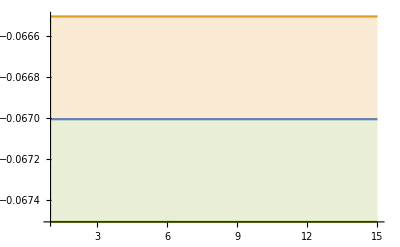

```mathematica
Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,15},Filling->{3->{1},2->{1}}]
```

```mathematica
SpoilHWFLOPlotN3=Show[Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,Length[meanErr2[[5]]]},Filling->{3->{1},2->{1}},PlotRange->{0,-.3}],ListPlot[{Table[{τSteps[[1,i]],meanErr2[[1,i]]},{i,1,Length[meanErr2[[1]]]}],Table[{τSteps[[2,i]],meanErr2[[2,i]]},{i,1,Length[meanErr2[[2]]]}],Table[{τSteps[[3,i]],meanErr2[[3,i]]},{i,1,Length[meanErr2[[3]]]}],Table[{τSteps[[4,i]],meanErr2[[4,i]]},{i,1,Length[meanErr2[[4]]]}],Table[{τSteps[[5,i]],meanErr2[[5,i]]},{i,1,Length[meanErr2[[5]]]}]},PlotRange->{-.03,-0.005},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]],markerlist[[4]],markerlist[[5]]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]},PlotStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau_{\\text{steps}}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3\\text{ (LO)}",Magnification->1.2]]
```

-Graphics-

#### QCD NLO - gauss

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={380,380,380,380,380};
NWalkers=200;
Nf4α1LoopBig={0.4,0.4,0.4,0.4,0.4};
aList={1,2,3,4,5};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
csvData=Table[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"],{xx,1,Length[aList]}]
```

({mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.28631645634615777, -0.2926427848825538, -0.2788712730442414, -0.2827749091679838, -0.2772202123068256, -0.27225120130549874, -0.2703861855402711, -0.2670106432001371, -0.2641327377182561, -0.2627337529263755, -0.2646526370361666, -0.2661402141457649, -0.2636316920627569, -0.2626299220495483, -0.2648837293367061, -0.26869056445728035, -0.27558219833653436, -0.27606960193296975, -0.2745625618209495, -0.2771431082892244, -0.27468828685919466, -0.2782936878492055, -0.28042225599660725, -0.28801723134838736, -0.28428423708907974, -0.2847831838304509, -0.2894588937508595, -0.29373227977134, -0.281191882392888, -0.2821914507620696, -0.27845234711504807, -0.27267383387733485, -0.2715755838859197, -0.27684609369222185, -0.2720987069341874, -0.27529606709865934, -0.27271255664920324, -0.2656198148107799, -0.2678162998603784, -0.2744103413897571, -0.2738072571517212, -0.2701988764491534, -0.2772464281318425, -0.2814293367528067, -0.2764413997461464, -0.2818745333608663, -0.2853473497520568, -0.2814719771009946, -0.2801026279766793, -0.27594905891682436, -0.28215907924989775, -0.27022107353495534, -0.2741482055165547, -0.2756102877496673, -0.2798323727029381, -0.28466219281066063, -0.2889647307999682, -0.2845913548768931, -0.2824253720967455, -0.2836980897789229, -0.2852147334143397, -0.2985157807793937, -0.2946589330234373, -0.2860755976572846, -0.2825074578445656, -0.2805503330721456, -0.26559641869057243, -0.26508107601437125, -0.2668754767903977, -0.26832339170992164, -0.2682457103217082, -0.26351229726371533, -0.27075480231718496, -0.27782248992891456, -0.26494968355234727, -0.26604327421848284, -0.27029131917210003, -0.2645474794807896, -0.2678870445080547, -0.2661126987488659, -0.26425212922134783, -0.2733186746607933, -0.2728578507867138, -0.2737133414357402, -0.27363890480696407, -0.2766950886259887, -0.28860969129117525, -0.29717165910459664, -0.30041758247964534, -0.29568946740801166, -0.2830875323062312, -0.29874810977305155, -0.2849549797600802, -0.2775917934244363, -0.28243248645166097, -0.2739936545786255, -0.2787501301770832, -0.2712260481389305, -0.28493166261280456, -0.28101071595779564, -0.27234276428588994, -0.26468059410997047, -0.2715776123091082, -0.2723164683247211, -0.2736945435190177, -0.2632435251808682, -0.262186818253185, -0.2677071468727247, -0.26582501690189736, -0.26619248264194983, -0.26759368500195335, -0.27054745608167396, -0.2800817780988647, -0.27967861834147667, -0.27539908070077196, -0.2690772751086094, -0.2688685655647894, -0.2893973191280231, -0.30277870957303377, -0.2791486574198038, -0.274612924012573, -0.27902166466292916, -0.28154239233665906, -0.2770944303714295, -0.27676052076060426, -0.2754815445880755, -0.2766940832705057, -0.28067129108467764, -0.2764968369634366, -0.2763366119308765, -0.2732693555263636, -0.2616397665824777, -0.2647495723365638, -0.2643964038745262, -0.26059056597805574, -0.2576628700767024, -0.25763113594143117, -0.2583314822728477, -0.25502984708841725, -0.26591893577748255, -0.2672128739065112, -0.27336849885271797, -0.26948012756187306, -0.26735071617689393, -0.2617931859328774, -0.2787994000679891, -0.2865519668505568, -0.28132333797431053, -0.2819382955380264, -0.30716003536096076, -0.29549866713841166, -0.30698451331372584, -0.2999913157252824, -0.2939048211706528, -0.29469892362107747, -0.29758783631159547, -0.31076264663110476, -0.3031451875222407, -0.3038474231838217, -0.29510789835922174, -0.28122523917592684, -0.29134522648140226, -0.2978882329273277, -0.2892330173971618, -0.2969079336723333, -0.31824215263433386, -0.30016346679506134, -0.275952485495742, -0.27461677048367167, -0.2734186073786449, -0.2720846854593335, -0.26858191455310143, -0.26935922571691695, -0.26712691413036216, -0.26366332916278246, -0.2683239424109996, -0.2586167537083802, -0.260302822875093, -0.2653292764394934, -0.2688783012953345, -0.2661709808331533, -0.262270295821968, -0.28289912410623896, -0.2737628876927096, -0.27179999339880884, -0.2748095793777102, -0.2759822582480902, -0.27621786296973394, -0.283184980853793, -0.28146268192951546, -0.28244410448051555, -0.2731424205662289, -0.27000186020023814, -0.2848345277575734, -0.28268367481984646, -0.2740119057421075, -0.2840922677061957, -0.2804637970594328, -0.27004141918083624, -0.2664092815778799, -0.2694363158415281, -0.2676675666596971, -0.2720592332560501, -0.27020090388878854, -0.26693859789214985, -0.2751501565608705, -0.27031764656543467, -0.2785001029209033, -0.27497844500424334, -0.28121585762845736, -0.2910544685579658, -0.2985685754108737, -0.302085226347072, -0.2984316263198625, -0.30456415343267274, -0.28458274991876464, -0.28342763803266013, -0.29309545861061176, -0.2843055507151305, -0.29205662410669925, -0.2851163589551739, -0.28102107841331575, -0.28532022512237665, -0.2797438067406569, -0.28033077204078954, -0.28537954658848774, -0.2806541343712279, -0.28448673514555506, -0.2958516577326099, -0.30462135299555987, -0.33019843024698253, -0.3051029265113401, -0.29827330958166454, -0.30806563522990804, -0.30437607800416416, -0.3002114156693345, -0.3013214787385064, -0.2862430751486137, -0.2890110761025184, -0.29709308385782623, -0.2893509611102897, -0.3014372413950333, -0.2922680531133999, -0.2822739461753031, -0.29712851389479933, -0.30628597734214963, -0.3118831210945402, -0.303604845451981, -0.3075522159840502, -0.3089210251551483, -0.30736404514793514, -0.3069959477774255, -0.3050775049441211, -0.31007348853127187, -0.30228341819101484, -0.30576791364410216, -0.2923154217891871, -0.29147438557703464, -0.2837658907558922, -0.2845647457143024, -0.29387679195295285, -0.2856991405780957, -0.27233713469533755, -0.27213473729183857, -0.2713771989691433, -0.26728386674221577, -0.2616437633460487, -0.25562417407720367, -0.25766154511324385, -0.26271094577083337, -0.264739850966766, -0.2655816849654641, -0.2737797077356238, -0.2631960914685694, -0.262360391529731, -0.2628461881872288, -0.2571227063075286, -0.25567537236898746, -0.25184981534908746, -0.2491265390817453, -0.2564876437727909, -0.26055368213718827, -0.25690629158061135, -0.2664566192392067, -0.2642662397829658, -0.26605221532152046, -0.2625010146071045, -0.26433682462419683, -0.2706895544948143, -0.26877009845054445, -0.26747897518055985, -0.26310350551570755, -0.26342263227260204, -0.2706402226399774, -0.27899093619043136, -0.27378805419378627, -0.27483801581662515, -0.27191612797767695, -0.2758659169151494, -0.2852893834859263, -0.290315824349647, -0.2937438901186612, -0.2979196706717137, -0.2950770687230045, -0.2951038604885244, -0.2906262296489472, -0.2828288109051711, -0.27994934040337033, -0.2780079236251808, -0.27926461461111973, -0.28859932959476786, -0.2876633660899865, -0.2826527906851827, -0.28139407637258884, -0.2840333527940998, -0.28427785774165015, -0.280098386785556, -0.27830270063037216, -0.28040404098022403, -0.28801571736127307, -0.3072366489024577, -0.2877084208288972, -0.2846337715046496, -0.2840171278491122, -0.2692305471326041, -0.2722085791033893, -0.2711594539223121, -0.2753761788110896, -0.26975480063752244, -0.2621506188951983, -0.2574813779051508, -0.25974405291206276, -0.2527040304655154, -0.2634483687242402, -0.27105359675538454, -0.2955315922604079, -0.2806723408864079, -0.2661116201258643, -0.2836646072869749, -0.28853008136560326, -0.3137550653553636, -0.3545123755452154],[0.012007718204898666, 0.018978799257939355, 0.00975879333746459, 0.012791311888857975, 0.0101088798018092, 0.0074937458724801415, 0.007441333269151143, 0.0068538509029466505, 0.006325303553463188, 0.007381375870952217, 0.006838639043723052, 0.009185995455797376, 0.007202446810081062, 0.005947014876812316, 0.006384292800908299, 0.007619989080775992, 0.009196128806161644, 0.009537698741323493, 0.007096000865358854, 0.010141312332483226, 0.007378833771410399, 0.007549254578686396, 0.006990915525306861, 0.010037296844086269, 0.008420519079708508, 0.010136259185991, 0.010563151090045086, 0.01564386164671212, 0.010757224165784056, 0.011223029440951784, 0.010426276048796363, 0.0070333971773128955, 0.00818046890320799, 0.010426923475325832, 0.007505428402863287, 0.007412102748110848, 0.006449941470087774, 0.004827856194396705, 0.005576974449929128, 0.006564324860270252, 0.006768183846734334, 0.006616693699909077, 0.009968093516667925, 0.012673827966838505, 0.009093301250992022, 0.010978519090180664, 0.011350943285872626, 0.01089725223239796, 0.011550915789619781, 0.013037049110998086, 0.0168267646665879, 0.00832449004343275, 0.008789557299307676, 0.008766746067297498, 0.010657821766744688, 0.013746655905172234, 0.01998740612123295, 0.015117186714696694, 0.011566208812556648, 0.01033916278600383, 0.010934774544871807, 0.019015066293613422, 0.019563252230004775, 0.012085442873076056, 0.01161501970917425, 0.010616783637966858, 0.0084256406006712, 0.010348371541484075, 0.013606823987505647, 0.011385865030028168, 0.006637087620312718, 0.006355088149091115, 0.009642588088968614, 0.012680483323833655, 0.008464457982164074, 0.009573402899184956, 0.012049258067149512, 0.00868302568651087, 0.009781421034511262, 0.008387534721237629, 0.0077727116095164875, 0.009063972046373436, 0.00908306680386319, 0.009094219444439356, 0.008632952554572287, 0.01080642598631834, 0.0172876060240442, 0.016352125290771735, 0.019636305593028525, 0.016795450232620013, 0.011342572089398074, 0.019592043864836133, 0.013115126735251406, 0.010794443633749333, 0.012693675639615586, 0.009540531520546394, 0.011148640578857052, 0.008609403633168157, 0.01642128704842704, 0.014987029213456085, 0.009443473374112808, 0.008093725095250815, 0.010712566019671904, 0.01289144747316813, 0.010743398874832622, 0.008175844234010908, 0.007854170109640877, 0.010720102049794008, 0.00884028703007279, 0.007999882108762919, 0.010166074141783443, 0.012238627886153229, 0.01645318956889808, 0.012891030635766404, 0.012012668992426362, 0.009004129490946932, 0.009952134305551733, 0.018662048754834366, 0.03200033383580321, 0.015223956117553833, 0.011242249156408687, 0.010765940653860199, 0.011493932995786903, 0.010998459969467704, 0.009970888608673819, 0.010510860936346029, 0.010572382856774606, 0.015732753349267718, 0.01387822279023194, 0.014266838769333899, 0.012530297396899943, 0.009340782532006424, 0.011147869032160779, 0.009261341485146797, 0.009848040474854351, 0.01040300718102173, 0.010536135389647226, 0.010818711991000297, 0.010203921336098577, 0.014719106511930629, 0.01552189381618826, 0.019277934986561933, 0.01591089215980287, 0.014330393477858415, 0.012147615304849832, 0.016509306761232103, 0.018961331740507695, 0.017661590847313467, 0.01919743733009551, 0.03596469009410651, 0.02851770152851864, 0.032251014212228674, 0.02773283943258415, 0.022392676838465006, 0.02428725579236324, 0.025611411234157767, 0.030234955739521875, 0.0317958909034706, 0.035021625381099944, 0.029576576489500874, 0.02000066225457195, 0.02605145401590163, 0.027540391213518263, 0.02560977019128509, 0.026986970935609065, 0.04518403791605617, 0.03211438569909096, 0.017062812998208405, 0.014249994726191975, 0.010095692399792093, 0.009493391595095173, 0.012935959637345248, 0.011736032958350991, 0.010115149297011114, 0.010768158861421736, 0.009662378668177977, 0.011454021225097585, 0.011301996527931344, 0.012361844749122799, 0.015419776014816717, 0.013971955537833801, 0.012889388526852797, 0.022807151989207183, 0.013846455701248421, 0.013643469328508276, 0.014197707647180063, 0.013662664306200825, 0.013838879321138996, 0.01496105076128274, 0.011401653802292341, 0.015691349518122254, 0.011563466450242005, 0.01017444840925755, 0.015676832831297238, 0.014059275217102322, 0.010689502147991815, 0.01693392165793006, 0.02144712489967248, 0.009972655941165958, 0.007967481353403583, 0.008310652155716637, 0.00788551897582649, 0.007505321284193209, 0.008211441940587965, 0.009089248821270646, 0.014422821486851945, 0.008556165270025057, 0.008643531089672783, 0.00807229416606051, 0.011511955306569623, 0.015100176013710389, 0.024295405532898422, 0.021725221234513297, 0.017379515341267807, 0.024371125049048203, 0.011800132389354996, 0.012000255965427408, 0.024618220694987973, 0.013149547030342138, 0.014705240344517652, 0.012038197510781973, 0.011114332736906875, 0.008984205342763176, 0.009716356294449632, 0.010051694008307348, 0.013319713580829413, 0.012183403662180696, 0.01581901739795999, 0.022800555563247126, 0.016366550177180875, 0.03228400695550424, 0.01868078968858327, 0.018339291776398255, 0.03247802534004314, 0.02810447787729393, 0.025158708134001465, 0.02770609992997739, 0.017916147499723707, 0.013976606938546883, 0.018204340568735357, 0.017110432820357038, 0.02762015039034609, 0.019540038943011536, 0.015940653955321328, 0.025049154062630096, 0.02763728987348633, 0.02572526506706888, 0.018539780052518412, 0.02218172190907604, 0.021125745186076062, 0.018285241519712118, 0.01822112312581488, 0.018512739973372036, 0.01877250190476414, 0.016974325813965564, 0.020320544597329116, 0.01563251024262124, 0.017719652752599648, 0.01806325865704898, 0.015033383621561095, 0.016530993447997737, 0.014844751507775738, 0.009230090532904144, 0.007846729476611067, 0.006557814610836261, 0.006705122210027834, 0.005722525280891937, 0.007392986439230301, 0.008522595461045829, 0.010240710186238882, 0.011976106797283989, 0.010174755233679009, 0.01227258543018307, 0.010896777353109476, 0.010135741389033618, 0.012071249714008575, 0.009278653845824235, 0.009380911964177594, 0.007541792230224191, 0.006987287626233819, 0.008152441062547984, 0.008396680369544794, 0.007463524309334685, 0.01017589263937772, 0.011012373038271855, 0.01014290700440705, 0.00987168547156012, 0.009143054816207823, 0.011032832774475233, 0.011882553415671395, 0.013443275694290656, 0.012678764052059477, 0.009772926634174065, 0.010332147514412006, 0.01567740205979675, 0.012271655171751491, 0.014675364674966334, 0.011707668107328905, 0.01518458634262699, 0.019302900723454426, 0.020028866270598456, 0.024237375720673374, 0.024193827589933554, 0.019333024152195642, 0.022131108273878722, 0.017420803154685003, 0.015132123452269945, 0.011095608347319073, 0.010461152203217198, 0.013662814402936223, 0.01394511711030602, 0.016310617497266512, 0.012476606833714687, 0.013204052387703502, 0.014992431849474075, 0.012474392095288406, 0.010236488724624607, 0.01098297648165981, 0.011647354459769433, 0.0150814280107718, 0.02899024108843695, 0.012754231671036497, 0.014280681025515702, 0.017659097236001543, 0.011895802552932603, 0.010120694635295623, 0.007518326872256941, 0.010579227423363508, 0.008413843893895568, 0.007495892314184781, 0.007146387374808745, 0.008822100265777011, 0.0072491468826750005, 0.011551314978112726, 0.015426096372277504, 0.03069808377129307, 0.01642029377367777, 0.010965694117432877, 0.01711081302863781, 0.01539297641511664, 0.022937309660215427, 0.04875546466914341],-0.265311,0.000916728,0.710799}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.20577373764907333, -0.20389285330279244, -0.2016497606824284, -0.20578063219739376, -0.20472349663282846, -0.2072779328931546, -0.2117555832790997, -0.21192725701318904, -0.21504212647832519, -0.2172068601226914, -0.21366086041564653, -0.211336563499061, -0.21175357688571167, -0.2091664530296884, -0.20781859095824914, -0.21223642831661232, -0.22433851482748726, -0.2350690371133582, -0.2283055192752486, -0.22020673588031708, -0.22205243060886753, -0.2181399243593209, -0.21379339150321208, -0.21967283114204875, -0.21735466075770152, -0.22028758079579178, -0.22686349960602317, -0.2286537874945093, -0.22978963616052628, -0.22929026740491795, -0.22927355352491527, -0.22916289440957435, -0.2301056247015711, -0.230003835933135, -0.22782757518275012, -0.22412089315617806, -0.22849578969040626, -0.24117245831191075, -0.24194461389985908, -0.2322209118135503, -0.24423192299642557, -0.23886963271536546, -0.24806935360435087, -0.24125088736105638, -0.24116228674610585, -0.23418166317460581, -0.2293877691266352, -0.23081632188065354, -0.23280807005088058, -0.23111651160848204, -0.22895035046408665, -0.22526456587295102, -0.22650818135620568, -0.2254655808828947, -0.22749154726502746, -0.23005055432601662, -0.23226354484175682, -0.23894810253962834, -0.23669121473865257, -0.23994346407628855, -0.2455612369352372, -0.2595175906339822, -0.24949827294234228, -0.23770280089730675, -0.23093478476869936, -0.2342387476541472, -0.22684194746455688, -0.22524004233553307, -0.22115777052758298, -0.22330015587335325, -0.2246086594475775, -0.2192621373282799, -0.22058224052614203, -0.2225463592973427, -0.22438261651055938, -0.21619434380263342, -0.21656397791409027, -0.21618018941165104, -0.21567464339993242, -0.21395464835821534, -0.20958205610483163, -0.20731084258242197, -0.20695867986253058, -0.20779205038324025, -0.206426778902746, -0.20763207294461603, -0.21012890679230284, -0.21271533236271442, -0.21295704771426413, -0.21750156729918851, -0.21707596409904964, -0.22292578077847128, -0.22079465819639238, -0.22200500585378, -0.21672033968470591, -0.21849612771790927, -0.22093837151402215, -0.22493956774230808, -0.22432654131082683, -0.22505612662773392, -0.22418931028718514, -0.22564046154350256, -0.22521068612201667, -0.22268135619165183, -0.2157494238235554, -0.21608905665578196, -0.2165972727282914, -0.21440762722078863, -0.21264121569180489, -0.21147334234541343, -0.20750911642076972, -0.2081085233680971, -0.208336772255115, -0.20281894697322186, -0.20271835550076417, -0.20498916402818793, -0.20876340282638173, -0.20760295505549353, -0.20042213592786595, -0.19499842952912308, -0.19281986742482082, -0.19176788729326472, -0.19202215050039118, -0.19402953238225074, -0.19353827889739153, -0.1978861561141106, -0.1953510496951838, -0.19736239000887446, -0.19648930555681984, -0.19643557332102077, -0.19514287952845147, -0.19605134388256285, -0.1965210613084635, -0.1945366451449401, -0.19375793700889968, -0.20147208572022207, -0.20628228273305388, -0.203586930001997, -0.20176674976486514, -0.20227260986737527, -0.2039565116564911, -0.20496858881905816, -0.20468842464993342, -0.20332736929342424, -0.2081471533640924, -0.21367461699984683, -0.20644757517722312, -0.20524890273261664, -0.20518994009396666, -0.20458181680130616, -0.2083962595644813, -0.2096875653375384, -0.20609690455866642, -0.21097883608854387, -0.20633480590252934, -0.1977654641195468, -0.19733063803327466, -0.19773749232038998, -0.20139695475553335, -0.19960079601018946, -0.20030451741251068, -0.20346922778701942, -0.21165376222067966, -0.2146778640342362, -0.20924199618485884, -0.21548602623344257, -0.21656801195470132, -0.21005686806949425, -0.2108443144990602, -0.21718143530407535, -0.21403962837522494, -0.21355461918413646, -0.2207193086727507, -0.2143686048018039, -0.2117768070483067, -0.2100416978635348, -0.2144920106424203, -0.21386814265342885, -0.22001245417528462, -0.2289588537696713, -0.22704643300531552, -0.22336237224141228, -0.22637018481771498, -0.22972002044680367, -0.23565435110966967, -0.23316766101421238, -0.23224728375622025, -0.22864015276570676, -0.22520739746683194, -0.2342843709969855, -0.21913996434239222, -0.21263099083895765, -0.23200210591783207, -0.2611992478716899, -0.24969857133653764, -0.2511947941981752, -0.25860303624454406, -0.26917684559729615, -0.2539495211387399, -0.23933496055647707, -0.23230046327775059, -0.24603370534332383, -0.24017929899157858, -0.23284705299879163, -0.21674656640128656, -0.21954723345139998, -0.21502743696861176, -0.22707318376494748, -0.22601833753999745, -0.23352271378610098, -0.24480845030930365, -0.22948877607825247, -0.24075676652155714, -0.24310496029916326, -0.24102730386914661, -0.23752596147121605, -0.2476766422389528, -0.23997614888397692, -0.2453934760867159, -0.24734303697392163, -0.2459480605071303, -0.26362162697339026, -0.26738484638728516, -0.26573308358636843, -0.26991814044233586, -0.24375135818619356, -0.24473595381938457, -0.2548871948500322, -0.25766473331829, -0.26566542265885085, -0.265217040157349, -0.2640494109841292, -0.2627915296690743, -0.2787423046148862, -0.26306348912522676, -0.261617556214332, -0.2881325697432802, -0.28149595734407395, -0.30992426513523963, -0.34074171792452723, -0.33666857357009156, -0.297312384264571, -0.27627693585660323, -0.27280305741559124, -0.2799446103838383, -0.30362913375629813, -0.2955632723553671, -0.2806844053305703, -0.26894293119493173, -0.2587048257513669, -0.25613208427067685, -0.2528376944533314, -0.2510844582909526, -0.2511008609910938, -0.2564847793723204, -0.24223346995159367, -0.24627125632358862, -0.23331251673903744, -0.23223304386810753, -0.25889172142336, -0.25208582846863153, -0.24188335090011148, -0.2584773643850178, -0.27032143954620186, -0.2693030803218663, -0.2944964785166168, -0.2932257046387161, -0.2957330634793208, -0.2990969679901682, -0.3074819300270148, -0.2957893660895428, -0.2955194056667148, -0.300142465415317, -0.317213865415462, -0.286900881964962, -0.30354376334422495, -0.2806725260335472, -0.2974263818997096, -0.2710388225101174, -0.27985858605702785, -0.2828390170971294, -0.29509946797253883, -0.29955705487281, -0.3102770628525951, -0.26508767743850803, -0.27678734917318143, -0.3150187086123129, -0.33062345126917425, -0.3248636030271906, -0.3027426384739895, -0.2882939586079191, -0.28162690682940555, -0.2657815930206617, -0.27816062958779186, -0.27449376369132045, -0.26668178961278394, -0.2526417013823636, -0.2501101147479151, -0.2617514477372087, -0.26749714230161614, -0.26937050844675453, -0.2582303879966575, -0.26431381728356756, -0.2698851534920762, -0.2757686572293206, -0.25490897973627336, -0.2541943592674423, -0.26589681923137953, -0.23394569699595916, -0.220217537076942, -0.21645555116336013, -0.22311951822411055, -0.2117951197282704, -0.2145525612094452, -0.22499175724493883, -0.22409143959866454, -0.2264136414222525, -0.2129139079794706, -0.215240938037655, -0.22950548383396177, -0.2313731529198421, -0.25903342917271305, -0.2742687656014278, -0.28038903902822665, -0.25141297252682715, -0.23641218170867775, -0.21407988428593622, -0.2133861655361106, -0.2004629304355011, -0.19632422715011197, -0.1994324820340761, -0.2051088200677978, -0.2041592854780619, -0.20151279618166987, -0.20815636898470577, -0.2069673266859001, -0.2056780865578827, -0.2126369189670072, -0.20834583430121556, -0.2190043416500653, -0.21345545624142637, -0.22770662420316828],[0.010201692510216536, 0.00901604611129365, 0.008544720501521958, 0.009414227627863635, 0.009023434434538957, 0.010451551082164714, 0.011529394844575552, 0.010964805442436915, 0.013449482283258743, 0.014811676530078822, 0.011209398504475958, 0.010873624046993508, 0.011846408024892448, 0.009617201911278581, 0.008285901635137, 0.010210262890090938, 0.01507920218504094, 0.021364406204950875, 0.01939796712921515, 0.01411043351851232, 0.014209486999024728, 0.010966033755282717, 0.008840261972542873, 0.010267539499389721, 0.008828160292190466, 0.008895735771596237, 0.01050375380410722, 0.01166059181288544, 0.011256071327046547, 0.010830401811197056, 0.011178472714491315, 0.01034224607897503, 0.012869889132839575, 0.012873941730598084, 0.01179197928843887, 0.0114065988271299, 0.012302570070457772, 0.016552405470722356, 0.01473575477929994, 0.012613915789392693, 0.01653758880259494, 0.015545128029731205, 0.025704482203648668, 0.01994338144806832, 0.01903760766566963, 0.015530792288032792, 0.013217346696843385, 0.012814457973443692, 0.014504107062709928, 0.013762423836107339, 0.014122907312726337, 0.014846314493672045, 0.014078257089008882, 0.01379458191830581, 0.01498016460395484, 0.017585877229253324, 0.02036795113155649, 0.024645435883995412, 0.023186796646361457, 0.024190670555885665, 0.024948867983180863, 0.029268827264809453, 0.023472683192779974, 0.01761360441704917, 0.016916856152673267, 0.016923791761194268, 0.015574135908963093, 0.015730023233940252, 0.014687000526343056, 0.016293470064234213, 0.015862678728444053, 0.01224334248021743, 0.014034701036100453, 0.013838491308765096, 0.013738537667527024, 0.01119077929930451, 0.011250561434122586, 0.01115567753312617, 0.011717864257744246, 0.011865629962456483, 0.010440946591404394, 0.010084549331621605, 0.008959016476477876, 0.010458495180670766, 0.010193129137995392, 0.009879923005098651, 0.011518474496053479, 0.010614410328996455, 0.01056574089321183, 0.012672570734709525, 0.011979115215329312, 0.01470120919676494, 0.013453610085739273, 0.012671331023920302, 0.010109632297775499, 0.012174621224161655, 0.012261987997906799, 0.016767386175158494, 0.014709935010527718, 0.013136546491340136, 0.013207417634979752, 0.013783630681426167, 0.014715331542040837, 0.013485774077775807, 0.00985961476509611, 0.009258485037633027, 0.009050108985079092, 0.00865070637942982, 0.007846558953897895, 0.006903730593834951, 0.005844418493193922, 0.0061492275040981184, 0.006785311877976695, 0.006959271479831588, 0.0074496942999320295, 0.00833064521241594, 0.011730834696594751, 0.011665960732015975, 0.00836714675539869, 0.006827450321702158, 0.006696352265574676, 0.005599849258754089, 0.006110189865517377, 0.006195681831195801, 0.0070248923398987416, 0.00871906026484311, 0.008129357963076043, 0.009313728035145281, 0.008228417954222538, 0.006774649920791077, 0.006851978850518565, 0.00636657478197008, 0.007229367866519874, 0.006926656356288836, 0.007086265204112139, 0.011383351270006174, 0.013828520729368032, 0.014428329756196675, 0.011890363240722956, 0.010110491155969684, 0.010860419808473331, 0.010978689588530868, 0.010840425068237482, 0.009913150846754606, 0.01068634689627904, 0.012458392149350845, 0.007558410115681939, 0.007259297823980478, 0.0065510361469904785, 0.007556851404232551, 0.008719521469238932, 0.009544201367730343, 0.009132338427559143, 0.011722803563368028, 0.008116830989303903, 0.005215766617557897, 0.006545016697161434, 0.006663327987943307, 0.008341134068307492, 0.007906478622736652, 0.00828583997252077, 0.011185392974194986, 0.014813966904724859, 0.015814631062846824, 0.011947131211228921, 0.01484031536268747, 0.013967573242690386, 0.012167171989576696, 0.01084859443238268, 0.01568090858948935, 0.012489151311187068, 0.01363717064205227, 0.016519482135818966, 0.012631298418892923, 0.012754795599360031, 0.009559545947057775, 0.012235381276943867, 0.011264079326109405, 0.014448727709522942, 0.02084229827395431, 0.01806372929902722, 0.017355010055867117, 0.021904091734136592, 0.022178103129389184, 0.023163411422539255, 0.021729843124341675, 0.022905823387711948, 0.0191858978997248, 0.017824829525886255, 0.02208860495929958, 0.012687281759679274, 0.011034153995560191, 0.021304996128718705, 0.04735654631920098, 0.03315315577917343, 0.025730099075509123, 0.03175245588341647, 0.036772245105472605, 0.027667188923921802, 0.019931658393557806, 0.018078681973748685, 0.026684372671952117, 0.023693690585636543, 0.021030872629144465, 0.01242015414142858, 0.014367607090185081, 0.013141771485933863, 0.017781219427492268, 0.017642299675159095, 0.020147150507889903, 0.023479443353862643, 0.01755324894376845, 0.0188763854509714, 0.021428368680107196, 0.019626261227250016, 0.0164776186729627, 0.02016742071559848, 0.017963425161039957, 0.017014963977588626, 0.018158811930248594, 0.018634832167788096, 0.02704480780393727, 0.03296272735836603, 0.03225798280372958, 0.03385133494748798, 0.018703431171723434, 0.0261426575463899, 0.02843908827904112, 0.02319137092874017, 0.02494008353891459, 0.02042111248284629, 0.024059576095166114, 0.025094610046918518, 0.024941969479481973, 0.020326721951577944, 0.023235052839410866, 0.029481383578700615, 0.029411052496842654, 0.03940290856548665, 0.05209219800989691, 0.05107234333894469, 0.03417473732458368, 0.03159048215581654, 0.03125357513253664, 0.03367560738944417, 0.04436864796538603, 0.03884233134840047, 0.02918053154649792, 0.024231522077944746, 0.01684654219960803, 0.018916771030778917, 0.019373097926463738, 0.0172090983826106, 0.018005439857068505, 0.021817497341206856, 0.020026802640708274, 0.024602036913050865, 0.019137763283937455, 0.02353244083759066, 0.042529448260115135, 0.037446481649565294, 0.03187330849719735, 0.046221604850055206, 0.04940109995587203, 0.05410095467870133, 0.07274161239127439, 0.07226442346827898, 0.070570207607711, 0.06672425159104234, 0.0721432282737447, 0.05524715042462871, 0.05287954968529231, 0.04968518893992872, 0.05733098923890984, 0.04147090158851085, 0.05804285210629816, 0.04069599697123146, 0.05759763348393591, 0.04096401816194123, 0.03929153551293818, 0.03524555655093829, 0.03474585452456893, 0.04746449078720095, 0.0524516155432965, 0.029346160230210153, 0.04100398454072538, 0.06892741356351181, 0.08150866362782776, 0.07926943320399409, 0.06774271176540382, 0.057562698184549295, 0.05537023744117307, 0.04571772879144443, 0.050700124679884266, 0.05108008513173783, 0.04599311617398203, 0.03754264720475661, 0.03802105545880047, 0.04164048232491592, 0.04305829424741677, 0.042340875497529684, 0.03413003325038132, 0.04169742723345345, 0.04274923431428343, 0.04785381367551954, 0.03646104783576889, 0.03601511431622915, 0.043625798804071636, 0.02729042800899236, 0.020712871202390497, 0.020198285733079385, 0.023248735964405527, 0.016890325266417944, 0.018488387023175745, 0.021064578690722122, 0.01951504720657508, 0.016045782564159505, 0.008605744373496624, 0.007440990061893437, 0.011356512881766301, 0.011937467002710008, 0.02595680250143197, 0.03462590791493539, 0.03939330682398329, 0.025309467210380635, 0.01680785042530659, 0.00809938237116352, 0.004756195347003475, 0.005263502293278781, 0.007144399443744629, 0.007157639383743768, 0.005547989858799127, 0.009144668529094246, 0.014660741066616023, 0.01750423533145184, 0.019062149857761234, 0.016427906126025207, 0.014519357037129046, 0.012207873781387074, 0.009646143668533332, 0.009422807437564205, 0.014232406845711913],-0.200104,0.00138058,0.402369}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.15554204604007127, -0.1546759487979732, -0.15538507605369767, -0.15300664539945955, -0.15474818017594488, -0.15663563136844919, -0.1573635865509971, -0.15855981231352315, -0.16315888029011053, -0.16879869070878686, -0.16556778743451686, -0.16699552762780545, -0.16946980506097128, -0.16817724476764676, -0.17039579430049107, -0.1695881773201672, -0.17160384162676076, -0.17255644485182542, -0.17663741813002137, -0.17769928911431737, -0.17235358859455693, -0.17206873436138267, -0.17223231394477803, -0.1748613289766873, -0.1719343165588736, -0.17257491032217015, -0.1751288923906088, -0.17682707526554034, -0.18156744645942854, -0.17884711991050278, -0.17854988589755605, -0.17466815813600609, -0.1724311714226185, -0.17456449285035958, -0.17743735022406396, -0.1763133717837144, -0.1805226937346874, -0.18300631563127398, -0.18376641463915352, -0.1870962490917492, -0.18543412615917548, -0.18658093123565694, -0.18361792375693925, -0.18581802399727446, -0.18994788462713924, -0.19026631482069004, -0.1877451807715257, -0.18962194146417669, -0.18315976169144343, -0.18545844046724808, -0.18336301008855313, -0.17975253186307696, -0.17921562211197456, -0.18087659755067778, -0.18235763386743856, -0.18388976968666831, -0.18267667004681853, -0.183232616249661, -0.18431220225012315, -0.18419953037945602, -0.1802121867419607, -0.18357959793407633, -0.18407285704150417, -0.1813977542734105, -0.18208246911982034, -0.18091047330298712, -0.18200967335129306, -0.1825961559467191, -0.18236832013485807, -0.18768456433930578, -0.19312481163365108, -0.1889095644086302, -0.18827972261162457, -0.18273858183551103, -0.18129054601180314, -0.17764071106827395, -0.18362401215789095, -0.18188320569680436, -0.18259377433422844, -0.18118936121048704, -0.17767279003777067, -0.18096116439056803, -0.1797344273713732, -0.1782170946207297, -0.17921433344723522, -0.18019154517296365, -0.1807580292329634, -0.18121291230385683, -0.18167091598034565, -0.18238368488677398, -0.1834237780387776, -0.18784788915663372, -0.1870284117943982, -0.18859378426112708, -0.18500436340797516, -0.18704464674417629, -0.18751113515517953, -0.1886026051784925, -0.1893536255133807, -0.1921656005466108, -0.19052807200367158, -0.18474668580748055, -0.1829680183634765, -0.1855592760008857, -0.1821621298509519, -0.18264146817852597, -0.1851682337609559, -0.18599118876949428, -0.18241151336089004, -0.18916464488414803, -0.18367990354038127, -0.18266218446220062, -0.18210617252240105, -0.17783815624093835, -0.1767581472513886, -0.17359839623522658, -0.17198577455665784, -0.17070575445926137, -0.17168716041320667, -0.16865454906024352, -0.16490461001973833, -0.16509797356754116, -0.165366184176692, -0.16521392633781284, -0.16423641536362074, -0.16411110972410256, -0.16563290313573614, -0.16278518575389833, -0.1631668656970545, -0.1648480303836687, -0.16294041100540133, -0.16328284378673102, -0.16366253370391176, -0.16657020817996543, -0.16954896959516472, -0.1710369243771685, -0.1700106343711372, -0.16831812885083627, -0.17157932224014955, -0.17287371933383516, -0.17764873895880537, -0.17738999677035394, -0.1736648549232566, -0.17552363905504753, -0.18030913095454784, -0.1831813185156474, -0.18149767217392437, -0.1812358383745377, -0.18228508006816405, -0.18086720569099757, -0.17962035058758946, -0.17748016553201595, -0.17482051804449772, -0.1749061814541839, -0.1744973572404054, -0.17301544546881364, -0.17272772056174415, -0.17059143667398086, -0.17145278354855967, -0.17066497268859487, -0.16999847807145435, -0.17160880237044424, -0.1739113166523131, -0.17427457872024865, -0.1772808714175675, -0.1772104092601824, -0.17832357405287555, -0.1743757447755165, -0.17423656846827107, -0.17449393727583423, -0.1756293791301149, -0.1753146754550645, -0.17856983589458922, -0.1785284581267853, -0.1749955843495811, -0.17921139234218916, -0.17961177919919538, -0.18040724692391275, -0.17857607049301194, -0.17431177294974617, -0.1775209612627891, -0.17315262262697734, -0.1702260884333599, -0.17143710643735902, -0.1701616220379572, -0.17046284740635734, -0.1681122594286561, -0.16889096600295078, -0.16880118088691437, -0.16773769845323752, -0.17122389235692018, -0.16900051837007518, -0.16816057460282965, -0.16723886944201963, -0.1693433469335293, -0.17392870110476386, -0.1724934626318693, -0.17465662839857782, -0.17252031013019484, -0.1735094775695198, -0.17140232904442623, -0.1719773121464279, -0.17238081381530826, -0.1692935211998045, -0.16907282357118789, -0.16834516741764868, -0.16787220144528028, -0.1691676533987195, -0.17044866019296978, -0.17361341165415975, -0.1731007971148558, -0.17292316664861163, -0.1733180973099168, -0.17361723085117592, -0.17552180055417965, -0.17499932648505764, -0.1744006104456711, -0.17578660568463644, -0.17864306119794915, -0.18011470368202923, -0.1799185744753389, -0.1788418099351668, -0.17935303453136725, -0.18256466529471924, -0.18316844621404502, -0.18474742853309364, -0.181820992928931, -0.18660761387129382, -0.1935223404200759, -0.1966376417159415, -0.19574058562962895, -0.1940307729496792, -0.1914387377633081, -0.19453692574754516, -0.19288079762100446, -0.1909714145841597, -0.18938628989250936, -0.19094952560446007, -0.19157285039381722, -0.1978625071506291, -0.19791646189792636, -0.19555424226240528, -0.19235914116127176, -0.19318464173094904, -0.1995133221702862, -0.19284757175994885, -0.19148605502197732, -0.19590150148725136, -0.194880555031909, -0.20102387659876056, -0.19708291094082994, -0.19440389173324807, -0.19270239700746128, -0.19437114103902586, -0.19623405954325862, -0.19229235531810632, -0.19744539741250886, -0.20422273888804426, -0.20038934547536277, -0.19624089827364777, -0.1977935086403906, -0.20668297114472092, -0.21382184672426946, -0.20543330716067143, -0.2177974031287701, -0.21210429984450882, -0.2169279221376322, -0.22684701416784034, -0.2198626306419252, -0.21628126612910664, -0.2273049705253152, -0.22192433070104678, -0.2136586577367111, -0.22137866044427493, -0.2270767375602161, -0.21825024790175368, -0.21354432840120852, -0.21282334310619974, -0.21618946657658908, -0.21744548182203688, -0.216982585347651, -0.21540047756939293, -0.21136677991793987, -0.2107890787431151, -0.21205489332111688, -0.21287787312585207, -0.21457063441760904, -0.21581872166283042, -0.2176554595295109, -0.21402638485272832, -0.2254285638159077, -0.2230585168723122, -0.23445379079241097, -0.23338662400566196, -0.2421248769934796, -0.23614748855425402, -0.2415241756353062, -0.25316632442967824, -0.26650360141405083, -0.2732733483290016, -0.27794083813674453, -0.2651320169271606, -0.27780433912850033, -0.28920067930324445, -0.28129206230189197, -0.2889716982642792, -0.2803445509741752, -0.27951803312920065, -0.2620055197258487, -0.25891498850610184, -0.237369058929226, -0.24310660044841087, -0.23895593502379744, -0.23294613663394137, -0.2307854086019565, -0.2338166609307087, -0.23619320283626666, -0.24227103532067626, -0.2429675329894262, -0.24810679234581295, -0.25600252022987724, -0.2530739380380312, -0.26570302877963753, -0.2486407833296599, -0.24800191408880223, -0.24764324569890886, -0.22954504360294192, -0.22437511753338138, -0.21974420168654105, -0.2196471057687743, -0.22327430934630532, -0.22413310860875335, -0.22530272036780025, -0.233291968227507, -0.23157924477565137, -0.24190053463581734, -0.23860081566143698, -0.23574310565661352, -0.23309588688954172, -0.2424921271990135, -0.23343841936228613, -0.23149548381664847],[0.00793415159660991, 0.00757860101807199, 0.007676013212613059, 0.0067492553916219545, 0.00756963449347661, 0.008342259866748428, 0.008404472417452792, 0.009027028849735563, 0.01147333389586003, 0.014516498431035791, 0.012386988396265697, 0.012633119117721915, 0.01427057002043067, 0.013243066446640042, 0.014005769149947772, 0.013069663220870035, 0.013648648439214582, 0.014175321881211126, 0.016349372191738917, 0.018046325240706894, 0.01297208616428119, 0.012612717262575915, 0.0125361399634493, 0.013271743900655926, 0.011815027576441551, 0.011444675880784447, 0.012078682975817013, 0.011455996176969591, 0.012764330064555145, 0.01213664731593442, 0.011849040041066098, 0.010690076307190086, 0.01021494551120156, 0.011175512365446163, 0.012550725745824701, 0.012175056469528366, 0.013769677645453213, 0.014632193195919276, 0.014517363420999258, 0.01572744832387842, 0.015030835145395233, 0.015375548104458486, 0.014013100947490798, 0.01487760364509366, 0.015567527063899012, 0.01569598895591539, 0.014280784179083905, 0.014688282581406645, 0.012564656249566533, 0.013824401287769322, 0.013414315037997681, 0.011874022120793143, 0.012316753199959578, 0.013057122673251173, 0.013501734725250165, 0.014553659693956908, 0.014395653752922956, 0.014020346700452999, 0.014043568927489205, 0.013100976562579626, 0.010651406021022288, 0.011404188198837572, 0.010750249132507604, 0.00996931192691668, 0.010431934023930481, 0.010350379104423548, 0.01058636451961619, 0.010679603356719738, 0.01075892666281291, 0.012664039139477444, 0.014473927506073767, 0.013004928350296964, 0.012498497412257814, 0.009984202875409028, 0.009356069766154572, 0.008089658368421623, 0.009540554938186008, 0.008940973168731933, 0.009295427017278089, 0.00865489455702195, 0.007718009192858962, 0.008152672120401824, 0.007539181151500314, 0.007239004625027316, 0.007544199765982831, 0.007762471068177014, 0.008711994748516446, 0.008278237097501936, 0.008488262491814594, 0.009125089554802818, 0.010220314545693774, 0.011915785259801949, 0.01082488673999129, 0.011022979910786853, 0.009125183920922044, 0.010439275004002654, 0.009785736847613585, 0.011305955655872653, 0.010936721824633424, 0.011113617756147437, 0.010449513918890261, 0.00816136605070781, 0.007549665775864806, 0.009168192838212236, 0.00816940144188537, 0.008387826699378213, 0.009487505224786892, 0.009273232062284063, 0.0076867399269919335, 0.010976099650365417, 0.008583396117863164, 0.0075711066670986924, 0.007192309941408279, 0.005738193752951557, 0.0057049316479961575, 0.004891507386832905, 0.005448080251599866, 0.005935708607184571, 0.006474214789830829, 0.005667492919103923, 0.004010778244428833, 0.004478528851621503, 0.004994691546020201, 0.004430667450697747, 0.004490795380911684, 0.004238309767015808, 0.005354998474903817, 0.004620419207368343, 0.004548423158698102, 0.004249120510418487, 0.00428286430542954, 0.004114839470534874, 0.004220362659943058, 0.005586338115007537, 0.006582051203174076, 0.005733798351085286, 0.005433792445752325, 0.005360086570516976, 0.007207892381473496, 0.00666960361302429, 0.008224680539690629, 0.007037876370013425, 0.006113840083984223, 0.006782789758962773, 0.007429484916754254, 0.009723034657509259, 0.009145456385282061, 0.008910976616026384, 0.008979052237342194, 0.008009046181472959, 0.00716229788734369, 0.00696602005840856, 0.006481428524198442, 0.006188087738669674, 0.005415183617338908, 0.005559257226821196, 0.005955617544526933, 0.005156794460533749, 0.005264091254032672, 0.0053667981787759965, 0.005385941140194561, 0.005844862478637592, 0.006026780995281938, 0.006374252782910475, 0.0070190440743001375, 0.0067908846135198075, 0.007114476728730287, 0.006973702441928365, 0.006863683774259557, 0.006954583563047525, 0.00825156900697015, 0.007687607280749347, 0.010310433367341752, 0.010386468244540857, 0.00804789353054236, 0.010997286407324253, 0.011291907406455777, 0.013251462417846612, 0.014221347086883088, 0.010988939347961968, 0.01385909306341431, 0.009340466516341829, 0.0068706887131306784, 0.008776017584465182, 0.007818604125639847, 0.007618837430134961, 0.006934393638218544, 0.0077132069330955065, 0.007001231523675825, 0.006692183788478673, 0.008961477293671782, 0.008406633219715286, 0.008564143979461654, 0.007304227154658865, 0.007775032767525325, 0.009031562411733505, 0.008161275847252528, 0.009072456613103306, 0.008199402084901846, 0.00847498565335267, 0.007614892708810589, 0.007145507320845358, 0.0065167378876775746, 0.006024723027578422, 0.006163817356349612, 0.006488980354064134, 0.0059829239478213685, 0.0062231201216742475, 0.007472038495444332, 0.007897644626477527, 0.008297885480536386, 0.007505277213653591, 0.007522801256221321, 0.00723623971214887, 0.007156719229026308, 0.006590493346611251, 0.006177051123236598, 0.005898529162720689, 0.006631548291669148, 0.006895678790749562, 0.006574436741957339, 0.006840509320849224, 0.006784318292755762, 0.007605665226056667, 0.007624788142939637, 0.00837669835045445, 0.007214032471063155, 0.008693695620933991, 0.011036830624464826, 0.014604855242781704, 0.01478611537076106, 0.01270629762844266, 0.012087004144276565, 0.012829177929993031, 0.013281382158815244, 0.01290639355505383, 0.011477334587181658, 0.011303938282384397, 0.010868421106265772, 0.013353058962808882, 0.012180495925550313, 0.011910957671709145, 0.010408164142612544, 0.009866773017977374, 0.01246125259286996, 0.009538930526967755, 0.008951645768988273, 0.00936593247379416, 0.009870337280730085, 0.012992914719323755, 0.011047657346058351, 0.012030628522174597, 0.011622061227330822, 0.013531674870040427, 0.016232295315135276, 0.014471290436231653, 0.017041253085956488, 0.023155288373894155, 0.0189856308844371, 0.014729044092339091, 0.01696937153487705, 0.02290653449217606, 0.02607836362098681, 0.019110927340585622, 0.02452343470292078, 0.021425100528701935, 0.023899110317726395, 0.03047141862120609, 0.027234741710458612, 0.026975829160573356, 0.03129388060595177, 0.02492462062050064, 0.019587686460494243, 0.02087406913856296, 0.02536785387232989, 0.019504371473004208, 0.01749169413724186, 0.016117880468274295, 0.015854011589819687, 0.01786922979281547, 0.018279133892541537, 0.018247975372308548, 0.017320294068460296, 0.01691896849415206, 0.0179917689545329, 0.015479980330912305, 0.018602688289135798, 0.01809904808043226, 0.018489145075325408, 0.017191935264948534, 0.020238246668408698, 0.021724248592907412, 0.02599484195782516, 0.02792657147908808, 0.03672047515458061, 0.03370792352254638, 0.03302997966427763, 0.03619356758625299, 0.04434689786563349, 0.044760612625459, 0.04697860504016167, 0.043914529800290716, 0.05238269582800733, 0.057994277382129145, 0.05413738812284723, 0.0524665228505068, 0.0559600068529727, 0.055268145798406394, 0.03750936171755179, 0.03638987081446118, 0.028244454833022004, 0.028834860431675977, 0.025611805185140845, 0.023826167647675575, 0.02133152354623425, 0.02221385589282913, 0.023378951378397052, 0.02289659763092752, 0.022501322511532095, 0.029349354653537402, 0.03738511987319323, 0.03958972860467139, 0.051547030030468156, 0.03589220053128387, 0.0346769008767312, 0.030899061133431285, 0.023807699626617666, 0.020963297837537028, 0.018153321479549085, 0.015546307183174816, 0.013844938178236978, 0.01413319528638184, 0.013419448990162886, 0.013436405198348125, 0.012878493760332375, 0.0149267412905986, 0.013074777356347501, 0.012504900100107212, 0.011537924721594832, 0.017528235560045097, 0.017958850608855444, 0.017866770076681877],-0.160453,0.00163296,0.767164}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.12345281057863143, -0.12274962910761072, -0.1235592227762263, -0.12254729587145746, -0.12341447748223337, -0.1233769531038078, -0.12476891609267486, -0.12490155506133618, -0.12737095776826932, -0.1290502717210918, -0.12825907416833057, -0.12968253641056968, -0.13074590270176661, -0.1318455810182425, -0.13242422699295395, -0.1329357325076414, -0.13311946576236544, -0.13313938050785448, -0.13474711217094676, -0.13387927051123683, -0.13552775878479664, -0.13553413192786784, -0.13603477054459914, -0.13746745083213083, -0.1392608199240046, -0.13877377981090544, -0.13933468983332953, -0.14015036556451038, -0.14170406695090537, -0.1418173548634961, -0.1424848054621571, -0.14553281157471754, -0.14621417805052958, -0.14282018231838195, -0.14021525398751813, -0.14074033586226012, -0.14239473255272098, -0.14474740475392767, -0.14478298295377662, -0.14836708804395538, -0.15463925633176503, -0.14841094018273254, -0.14954681016822888, -0.15053603166043575, -0.1461330709238346, -0.1483713907217414, -0.15132242677812419, -0.15459180283256696, -0.14995501571328312, -0.14890323970683766, -0.15113222155703063, -0.14986553306780573, -0.14885455662837113, -0.15065459595105843, -0.15628399962431128, -0.16290968055087982, -0.16009066043262105, -0.16340739741704674, -0.16385105285998658, -0.16190903170854118, -0.15705471818171082, -0.1588173938590167, -0.16005792642808098, -0.16603959768341273, -0.1581373208346568, -0.15704084874692328, -0.15663239324913625, -0.16095399336542934, -0.15809593573691147, -0.16166771254937876, -0.17276576837297705, -0.16390151816495332, -0.16225145494021057, -0.1623710061145438, -0.1627483690624431, -0.16163242930612373, -0.16528206091320036, -0.16678807517113264, -0.16642843241368585, -0.16307191906581725, -0.16207474287852022, -0.16842108107889606, -0.16935909371152577, -0.1674131436431791, -0.17781673711256174, -0.1720485358391559, -0.16577830912967387, -0.17194801370342166, -0.1715951643328501, -0.16275307268098108, -0.15869796768854375, -0.16556929791810324, -0.16547094455591077, -0.16164534985707218, -0.1663767508129827, -0.1622409563485172, -0.16536965460111475, -0.165242441081678, -0.17188850396955746, -0.17959799103443683, -0.18820375358256416, -0.1762361714016784, -0.17936297051618488, -0.17473877216870784, -0.17098877694896175, -0.17003770152653908, -0.173273762479602, -0.17071623526131088, -0.16546739776370437, -0.16298427037151206, -0.15982086187226685, -0.1573843210440996, -0.1575166613817383, -0.15536585720817203, -0.15627923952278183, -0.1522939890216537, -0.15094618751193886, -0.15294008201562814, -0.15336369658493387, -0.1527486841387795, -0.1484899889385853, -0.1482119845287274, -0.14837964740643078, -0.1467776228599823, -0.151473493654863, -0.1484969510989601, -0.15165491669681644, -0.15003437114224172, -0.15043443327804085, -0.1502809597845298, -0.14700635973016274, -0.14799935292882013, -0.14730672848271512, -0.14985789040607123, -0.14873428761439758, -0.1470163946942546, -0.14857829486502422, -0.14731357682444543, -0.14458955661087006, -0.14458278199651167, -0.14411206048103553, -0.14533593462685512, -0.14350070169455612, -0.1444651018942967, -0.14628185732429053, -0.14786196734535087, -0.15029986027956915, -0.15036565463857643, -0.15103526995408195, -0.15511699175129365, -0.15153266113902086, -0.15113001644796653, -0.14882097913097478, -0.14764310397058686, -0.15066760567116066, -0.15244489791499563, -0.15147148676523003, -0.15322775881890835, -0.1522570458513028, -0.15113933317744407, -0.15143475616121801, -0.15233523271038854, -0.1561174153371933, -0.15787690082588074, -0.16081207394203614, -0.15712307905590314, -0.15648313255736213, -0.15559490726353511, -0.15784154370860054, -0.15891297916638028, -0.1590113615737883, -0.1603804015756367, -0.15481843854142965, -0.1550562417233923, -0.1525483732008667, -0.15127589485694354, -0.14857339056773072, -0.1463031477837173, -0.14972114211799772, -0.15107071187519414, -0.15151613843962963, -0.15137319502339938, -0.1500267734431715, -0.14954876280220253, -0.15171725064397526, -0.15057669083197725, -0.14644082689059618, -0.14471433741947987, -0.14528291839226146, -0.14861763679981624, -0.14555374496490361, -0.14578413463885445, -0.14588039531345773, -0.1488471462029993, -0.15148553342516158, -0.15545717673706427, -0.1541535006839544, -0.15555178380993626, -0.1541451622897999, -0.15444912591532847, -0.1559020403552531, -0.15729309789855245, -0.16025792406818154, -0.16045095966367345, -0.15572970585512902, -0.15736390637483025, -0.15481123060425037, -0.15418831759355967, -0.15165428383078802, -0.14912192725457832, -0.1484408083503731, -0.1513374579723955, -0.1602857519571461, -0.15373741887558887, -0.15304652749437775, -0.15132202982747378, -0.1588362577681068, -0.15305394956059057, -0.15483601104648634, -0.15419796720285125, -0.14851182984731526, -0.15221418949827709, -0.1548237575286135, -0.15954123591707947, -0.15714576158504914, -0.15662041181157105, -0.15498871104179918, -0.15525055491343293, -0.16752845208810085, -0.1685738918695927, -0.1754332314876624, -0.16951165875270674, -0.1689407146837848, -0.17191556178181094, -0.17262959426475769, -0.16066174456683366, -0.16485856822271464, -0.15377652936795538, -0.1480606153487481, -0.14459353565333743, -0.1463644913544725, -0.14579240483575046, -0.14245276055045789, -0.14211148647942956, -0.1384852807025578, -0.13890992161936697, -0.1416764397657247, -0.14325066383827137, -0.1461200730585849, -0.15003184886988064, -0.14827232387403722, -0.1533739735202319, -0.15440226247381295, -0.14934533182634818, -0.1523935487324328, -0.15113186983974322, -0.14478806549449777, -0.14957722623475667, -0.146200985906411, -0.15264061873125573, -0.1486590015470461, -0.15012132561998195, -0.150354008490762, -0.155330719464967, -0.1565744134683048, -0.15740631523839593, -0.16090145663919242, -0.165982622482858, -0.16704135462606856, -0.17263767048402218, -0.17844731244387133, -0.18288153433371823, -0.180958324427703, -0.17888363020126113, -0.173701295227979, -0.16871168247292692, -0.16666579641145104, -0.16978120548518713, -0.17101320153958852, -0.1720766526178035, -0.16951263644469447, -0.16653920499259536, -0.16727368092350461, -0.17057870728009497, -0.16375913663991454, -0.17048386724609238, -0.16549220890456667, -0.1715310566942779, -0.16977198417604902, -0.16654784784513538, -0.1688618776473411, -0.164095895626634, -0.16305994404767302, -0.16331190449184455, -0.1709889476799327, -0.1712929123609883, -0.17225403258802816, -0.17506553852225448, -0.17580026417052125, -0.17162893753147657, -0.16701196242636518, -0.16716520994766493, -0.161902370575368, -0.1601810393398852, -0.16144260583561487, -0.1594644299057084, -0.15357365382770677, -0.1534028635415287, -0.15146452945131839, -0.15149905000190814, -0.1493167816385215, -0.14730508359996786, -0.14891862746889453, -0.14802379453798428, -0.14737710948096994, -0.15027231154349815, -0.15024669554496323, -0.14931646855857253, -0.1521052179456857, -0.15084639538667707, -0.15419863731735428, -0.1491495172937034, -0.15053965537269426, -0.15640593127818844, -0.1538329331409969, -0.15576010564251758, -0.15017302957800072, -0.1523061276843995, -0.15119599958673305, -0.14850691585420617, -0.1490998061083523, -0.1510033878761523, -0.14905582715887217, -0.14692351142635607, -0.1453050009568028, -0.14705502217186592, -0.14658702803748133, -0.1497120304387802, -0.15259068099820963, -0.14835064973693254, -0.15123665787636145, -0.15312783107653527],[0.005510020999766069, 0.005135721670143524, 0.005406817196663888, 0.005080249596575343, 0.005339805161247871, 0.005263330229428093, 0.005816094552514953, 0.006042918708121175, 0.007015230576680672, 0.007247752855818514, 0.006879044675815503, 0.0073250728102937975, 0.00783021290672969, 0.00810370106153762, 0.008553374314677923, 0.008661509409876533, 0.008861049620683268, 0.00830824473723298, 0.009047851632403134, 0.00865186236995687, 0.008697518414926136, 0.008629005251522033, 0.008754516104986055, 0.008772092659159729, 0.009276563756772618, 0.009058344332261818, 0.00903279924340662, 0.00923068598381938, 0.010213853441207312, 0.01043822704431248, 0.010694782712097797, 0.012247698289050478, 0.012912489943385896, 0.010751683833146116, 0.009353219999633528, 0.009927349653406288, 0.010616299913496621, 0.011654442109083105, 0.011889504375158214, 0.013620931629223716, 0.01763088723261523, 0.014170958250563862, 0.014331920695355676, 0.015269369251702938, 0.011868772142618738, 0.013385903735381793, 0.01597061887426505, 0.01833944968805124, 0.015129354232711027, 0.013124247818694326, 0.014218152115404541, 0.013586740642758405, 0.012806260374440302, 0.01285500068761924, 0.015768529655943928, 0.0194822760870012, 0.015341288681927261, 0.01736727732180127, 0.016867343782732698, 0.015876563182607252, 0.014448714874087156, 0.013769709398846166, 0.014361029909199852, 0.016160471540424274, 0.012960964644805345, 0.013009826901970589, 0.012748339717229636, 0.015787089280626228, 0.013594934458014407, 0.014147314325235421, 0.01990542481203748, 0.015348070239410233, 0.014032487509395319, 0.013423248738356656, 0.01381496576176409, 0.013307913574072404, 0.015436060181458095, 0.01651943114736773, 0.01502477825432459, 0.014238204109421443, 0.014869988209738325, 0.0167224804605684, 0.01642903859581711, 0.015395952861100046, 0.021153644702839366, 0.018087631977432406, 0.01407445540065812, 0.01652501430616839, 0.01756567543564972, 0.014624063233019487, 0.01269898783654882, 0.01666927403872458, 0.01555653663996168, 0.013312100460530857, 0.015595662801554224, 0.01302535193091576, 0.01346406000788134, 0.013815502603661982, 0.015573789376529123, 0.020215527066368998, 0.02417123220630583, 0.019894577513013358, 0.023588544107130124, 0.019608276066123465, 0.016511771603861827, 0.017268230967743062, 0.018343766994324228, 0.015810581441164328, 0.012015893948123116, 0.011153385189394188, 0.00980755773520522, 0.008050654347813746, 0.008299320238295825, 0.006864712321254489, 0.007041687165384642, 0.006153261120295784, 0.006088614126820872, 0.007001281521437474, 0.006672612220713727, 0.006313909123822273, 0.0057072371360021145, 0.006298216602037246, 0.005646286105933663, 0.004882399212497294, 0.0065698469333436964, 0.005896229481190624, 0.008637003871762278, 0.007497248856384346, 0.007303659014394254, 0.006160122371589717, 0.005319594483709665, 0.005501460322763061, 0.004736161197201294, 0.005257460387145421, 0.004668050018073935, 0.004150029532543869, 0.004602815843260327, 0.004298952255749184, 0.0038009403555882746, 0.0034415416317078538, 0.003592024534867687, 0.004079695262739393, 0.003878876831924684, 0.004891838440596567, 0.004825156114650197, 0.005042900456598167, 0.005542533726097121, 0.005180231080170718, 0.005312893804893054, 0.00678041202114098, 0.0051101133049939965, 0.004867640264826566, 0.004483340281273136, 0.004689324292674527, 0.005774489003499557, 0.0067849764718880415, 0.007660234099134681, 0.008605437941955564, 0.00782050859848795, 0.007961696355901587, 0.008713612503174253, 0.008687913726928323, 0.009301518933682468, 0.0103614919594733, 0.011706146134624793, 0.010054006787328817, 0.01037863839231908, 0.01105507496674018, 0.012648476417812438, 0.012446718110040337, 0.012019452440284009, 0.014016032494367985, 0.011286782848572945, 0.011737578876155397, 0.009956149533725962, 0.008641964862869495, 0.00725236816272233, 0.005462994813196387, 0.007689201955900624, 0.008425461978625235, 0.00810205235702933, 0.008046055796339898, 0.007245436123649969, 0.007368331407550177, 0.008103731789705195, 0.007686541638914072, 0.006408818406620129, 0.0055116113177158385, 0.00572536239616708, 0.007319912129005822, 0.00643229996719638, 0.006428465647648099, 0.006578482511539984, 0.00681365629068111, 0.007678632239050565, 0.0103333550365109, 0.008604489356766746, 0.008971126030855718, 0.00868552855473905, 0.009837608510549684, 0.009601404176815617, 0.009476024074465588, 0.010424268325246809, 0.010009883223625575, 0.008463786119933075, 0.008945296976778459, 0.008008920222838913, 0.007575301919665319, 0.006869943900399391, 0.006692449225076178, 0.00617099328296686, 0.006658817243288197, 0.016063116297791124, 0.00926771636779443, 0.009189832166826775, 0.008631462676390023, 0.011068976572972752, 0.008103478643817644, 0.008721903222481418, 0.010861005494227758, 0.007454413482603407, 0.009075905106418298, 0.009385116073310858, 0.011873497510570147, 0.009850916897009945, 0.010048410139497962, 0.0089880763495552, 0.009010126247729785, 0.014215086173029518, 0.015984404885257427, 0.020050875782005394, 0.018091161386927797, 0.018377494953308142, 0.021589009793081617, 0.02300667924059452, 0.016120488907055038, 0.018829628416355465, 0.014191779132394028, 0.011294112225132673, 0.010526068337788333, 0.010686167554446022, 0.009103124529377622, 0.006926271290115227, 0.005684144035214419, 0.004731555898088621, 0.004092691826434786, 0.00531416957896633, 0.005859138806132827, 0.007977901396280667, 0.010036769056023616, 0.008973009763306013, 0.012353926984538815, 0.014153386025354658, 0.011871536359232326, 0.011896653083649145, 0.010794825238279205, 0.0077219777417905444, 0.010080692400880109, 0.008351567843977477, 0.010552261342067219, 0.008889207515723904, 0.00791086352946906, 0.008381982698937002, 0.011376317930392687, 0.012538608622312673, 0.013430010127445631, 0.014865402572911704, 0.01718355231978396, 0.01591226330297341, 0.018616553220344903, 0.023369172206096828, 0.02493208107094831, 0.02307864864165676, 0.02180044675101934, 0.019011191574198814, 0.016025628038901778, 0.015856893516183777, 0.01578254086953736, 0.017346964133298, 0.018091260843584565, 0.016169018897412613, 0.015025782202086524, 0.01572107290401169, 0.017015019455799904, 0.013333141442332235, 0.01646124378892045, 0.013509604518903748, 0.015579041983686644, 0.015871132395883503, 0.013452984380351696, 0.015208975645746031, 0.012726436561375197, 0.011740213198744834, 0.012645692530904064, 0.016286882526044707, 0.015901955595853286, 0.015943609253544957, 0.01859508498575818, 0.019462590047334725, 0.017082559415690694, 0.015672708743843234, 0.0169025684951498, 0.013982290440236383, 0.01332745145021609, 0.014544926549199833, 0.013858533267908148, 0.009929880288753185, 0.009021574158695091, 0.00869221120597032, 0.008173670314082176, 0.0072968677590213825, 0.0068055868253493286, 0.00687672046253281, 0.006880795151855365, 0.00711480729533071, 0.00764400018558888, 0.007398841017197696, 0.006753886132892043, 0.007495577572326657, 0.007256524924061598, 0.008656662078909241, 0.00712615924631718, 0.008025218756715061, 0.011227067373817326, 0.00971636677349655, 0.009542312670054924, 0.007387918320215605, 0.008573084938541496, 0.008082531550901162, 0.006907996794707556, 0.007554112619366146, 0.0083856332559772, 0.007208761631061028, 0.006722120742272214, 0.006230016063861746, 0.006893947779972245, 0.0073731585868551195, 0.00864815608873731, 0.008971722041775647, 0.007970750567625312, 0.009056969592093827, 0.01000526703899596],-0.137293,0.00107775,0.495102}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.1029217862967891, -0.10306339560967538, -0.10356116880213233, -0.10567863152388861, -0.10718664660764331, -0.10475244493446012, -0.10514463741248542, -0.10538374820319193, -0.10529781083211837, -0.10522928010325393, -0.10558323865480586, -0.10604749550498825, -0.10620090517720789, -0.10687075083192053, -0.10754261146825121, -0.108327782333098, -0.1093572354826396, -0.10981686145459835, -0.11010319304147033, -0.11130469521934838, -0.11606510691393647, -0.11351245187598771, -0.11484948243314937, -0.11454050608141116, -0.11657916646686241, -0.11631327656519773, -0.11679182647188596, -0.11508695418625063, -0.116195179081921, -0.114870778004098, -0.11422234816812347, -0.11497141956346159, -0.11718602723281181, -0.11650612954074192, -0.11692827796644686, -0.1174426708828649, -0.11667823691842444, -0.1163857005856523, -0.11882089657293733, -0.11799676359791703, -0.11908189445639172, -0.1183373981244616, -0.1205702986003931, -0.12158383697016924, -0.12174664312873791, -0.12140465574570165, -0.1202525379272763, -0.1192522803887465, -0.12085725189888048, -0.12142418036025751, -0.12291276466176435, -0.12160539966285146, -0.12286934866348781, -0.12353706610848342, -0.12366120174462178, -0.12477496057202729, -0.12828316570032483, -0.13247293843993188, -0.12937232340154667, -0.12877111077294323, -0.1269423182244426, -0.12882433850773606, -0.13060281527296722, -0.1323208131869301, -0.13339769870861665, -0.13324852878763, -0.13069702003327607, -0.13102483272609733, -0.13287495519361286, -0.12991797891062584, -0.13057137137198468, -0.13021474660601565, -0.13134888335160858, -0.13188412676489092, -0.13407068855402285, -0.1360321449644903, -0.13713252328589853, -0.13404076256552036, -0.1344331606047032, -0.1314140913199244, -0.13068566253700786, -0.13343485662744192, -0.13305706693717836, -0.13358390324427283, -0.1337720240386915, -0.13322184537503143, -0.13414581630961914, -0.13586554680237317, -0.13747545318143733, -0.13599010994526567, -0.13642965521963737, -0.13871875651519186, -0.13903321807881389, -0.13758351394153748, -0.13875806761342652, -0.1371373108336406, -0.13761300106439964, -0.1368386477985834, -0.13972600303671107, -0.14321256429517087, -0.14587027741471276, -0.14475053238846533, -0.1452066037900607, -0.1417634611122088, -0.1410910559140758, -0.14182789415977598, -0.14401920993373232, -0.14300341568535302, -0.1401963434128224, -0.13814764640197133, -0.13637720116822677, -0.13413187776710533, -0.13397392283723625, -0.13154101184635678, -0.13381932730026638, -0.13211125786860084, -0.13209048816718133, -0.13187816201812294, -0.13155045662318332, -0.13040591857237116, -0.12993499917228096, -0.13108608593677806, -0.13120395016742342, -0.13037090598747167, -0.13203075262145963, -0.1348020307993159, -0.13604201355165008, -0.13499061119711978, -0.13670603137400236, -0.14207834138174633, -0.14555445127257688, -0.14862308136091065, -0.14687337447356313, -0.14557673445957237, -0.14472173702506452, -0.1432117481814742, -0.1406192377207333, -0.1378686200712264, -0.1377570687880708, -0.13805167710776117, -0.13796334178968045, -0.14065646239796362, -0.13954894196217296, -0.14025023076684867, -0.14484477096548315, -0.142028121821223, -0.14042306184204817, -0.13846002966573787, -0.13603836835897928, -0.13689846657617682, -0.13600243105219315, -0.13835609975118085, -0.13597962194537538, -0.13744185960290756, -0.13764557189061802, -0.13829980101233155, -0.1383060681844061, -0.13951390743692352, -0.14029052130741895, -0.14099578335279428, -0.13964235754596765, -0.13858476747563073, -0.1404794540292182, -0.14207048208041836, -0.14426588890319428, -0.14497188308312758, -0.14468772966643997, -0.14134178518762308, -0.14077014462509144, -0.13993062560482916, -0.13987239759862033, -0.1404888124031355, -0.14171224957729353, -0.14200152164361526, -0.14265431947032145, -0.1425669727219637, -0.14440323430785035, -0.14191239421320448, -0.1423816214343373, -0.1412529408586051, -0.14245253467995128, -0.14122214953175927, -0.14195036556695545, -0.14330953986989547, -0.14481375050601275, -0.14699534611748483, -0.14657874538175833, -0.14656609553204225, -0.1449817983150408, -0.15001032799591066, -0.147443735275397, -0.1492402193563652, -0.15034655648999523, -0.15217402291845736, -0.15189408845357477, -0.15510006109347596, -0.15247585283309859, -0.15180991666956398, -0.15345586340087722, -0.15326008636044325, -0.1507096973106669, -0.1518166790116586, -0.15239364339639289, -0.14940903263880595, -0.15062850956578688, -0.15170133393554017, -0.15008735178274507, -0.15095020461896888, -0.15162810344887948, -0.15070064030029023, -0.1501988015139719, -0.16086753170328602, -0.15752929761252138, -0.16442125702857704, -0.16095698578404002, -0.15909482407511036, -0.16317130166890217, -0.15372594304124412, -0.15335814410230372, -0.1585629967272171, -0.15462156847026037, -0.16353534714512422, -0.16929239767310833, -0.1686170547456442, -0.16414832286739758, -0.1679134523653217, -0.17064719342002252, -0.1692356098988081, -0.16003706669136722, -0.1537305707808056, -0.15177963124799168, -0.15535353598853863, -0.15712743309550473, -0.15716825125800962, -0.15196186693430452, -0.14926428635139913, -0.14841924265984768, -0.1448303209190063, -0.14626238628236998, -0.14646716887750358, -0.14963684207569736, -0.15246706297023369, -0.1454769896829392, -0.1475437744629002, -0.14622329465517386, -0.14855423962472505, -0.14786402442459926, -0.14769431485968856, -0.1515530638429322, -0.15059931322758113, -0.14918825428606292, -0.14854198506775207, -0.14620314572938567, -0.14328790774147743, -0.14285324186246157, -0.14280128612627746, -0.14303477026858694, -0.14507205201484583, -0.14561142748005837, -0.1442654485143664, -0.1446262844090243, -0.14852208666654182, -0.14907112444759962, -0.15101225187836204, -0.15102700315589235, -0.14937683697953894, -0.14983636028049915, -0.14873269618326831, -0.1486863993243944, -0.14981370282891815, -0.14937376371662986, -0.1508350752375091, -0.14766418755317218, -0.15164610900368425, -0.15388410231201055, -0.15053832947412357, -0.14595736634423734, -0.14720191016901923, -0.14510079244513605, -0.14977939470909551, -0.1531777510792589, -0.1536268067199386, -0.16217991201819712, -0.160051814313539, -0.1577507048647158, -0.15637063912347962, -0.15326520632264118, -0.1516803935471228, -0.15047094750933315, -0.14961326835826003, -0.14884954912659498, -0.14745994620469072, -0.14562801032603212, -0.14411106560268125, -0.1463507996110112, -0.1474724579263132, -0.14582571378721754, -0.14679312933692992, -0.14733088829580707, -0.1457436755987599, -0.14588439433612102, -0.14629457189336476, -0.14568254356093976, -0.14612871579839418, -0.14502728770187606, -0.14261132389082654, -0.1425964563886238, -0.14200979554804663, -0.1428821023129349, -0.14340924052099252, -0.14336963132597405, -0.14370230104061787, -0.14486328857874453, -0.14419689072305567, -0.14578938303577013, -0.14720474411919807, -0.1471844451373422, -0.14782058132831954, -0.14765862691275403, -0.14884618525113108, -0.15041117815402044, -0.14964641119849414, -0.14897918911086885, -0.15232865484021763, -0.1516175285885822, -0.15034712020791496, -0.1488232368675858, -0.1506496989460518, -0.14974817143871186, -0.14691240816909545, -0.14700527837199356, -0.14790961576985587, -0.1474322497570756, -0.14656612178303308, -0.14357972521059179, -0.14584320031270412, -0.1462491318740758, -0.1466596266986221, -0.14730288529326693, -0.14820731094853073, -0.15406648708660253, -0.15538561722287209],[0.004656633575600065, 0.004567905892648122, 0.0046891265449795485, 0.005902279906199167, 0.006256274809262619, 0.004824646848277956, 0.0048337300681144755, 0.00477812601939588, 0.004809301524714025, 0.004646063870014782, 0.004761554226393374, 0.004799050461019095, 0.004820197748237272, 0.004965115561305454, 0.0051633280166840856, 0.005319595668359137, 0.005558738308182562, 0.0055579564345208405, 0.005657957478085472, 0.006642059094138208, 0.00916955554144698, 0.0067989740048064115, 0.007423874147065841, 0.00678934103207923, 0.007752009352152144, 0.007097951022767096, 0.007202910551106239, 0.006548609942748489, 0.006892441927711122, 0.006392634469725062, 0.006235357833450392, 0.006836042656824839, 0.008129264362760196, 0.00765635772820377, 0.00781373264152577, 0.007581548498519013, 0.007082993431169058, 0.006916246868513666, 0.008249670995446871, 0.007316591051353695, 0.007329214364978845, 0.007098403802178672, 0.008021261548433698, 0.008437587818221785, 0.00829593437157935, 0.007840583785797408, 0.0073879443618845055, 0.0070615712252175, 0.007568697032208482, 0.007644592270342537, 0.008056170732308559, 0.007572630261130049, 0.008238358937791086, 0.008459038859603902, 0.008039993929329078, 0.008266072583948344, 0.010339035285306053, 0.01311318727774713, 0.010675101892423456, 0.010038631013548118, 0.008456021376943892, 0.008937793353035453, 0.009427403961351841, 0.010284937017024832, 0.010577153221789549, 0.010461843761328733, 0.009561913467657748, 0.00924781836356612, 0.00936129556846746, 0.00789942972701835, 0.007873609773473799, 0.007513398715488356, 0.008219687079670676, 0.007998786312726654, 0.008492842759772438, 0.009720569226790996, 0.009643027111488527, 0.008607488227256087, 0.008550884518968764, 0.008001265331190993, 0.008063106246363139, 0.008797987949118296, 0.008122190897703375, 0.008441978565280046, 0.008296405665945148, 0.008049948877669608, 0.008382001552542604, 0.008826767476144633, 0.009155060654848857, 0.008480929602669534, 0.0084794260886231, 0.009762334272034347, 0.008718544377367465, 0.008301157837993671, 0.00909527752906325, 0.007838952408023847, 0.007668891657544152, 0.007613549404734215, 0.008395308470985713, 0.009319028300239516, 0.009958133928178764, 0.00890938901315661, 0.00934875113483426, 0.008659410322008641, 0.008348831591768484, 0.00918654482496916, 0.009640068497731849, 0.008612304486650653, 0.008818487694617422, 0.007964612360712903, 0.006773267346620552, 0.005831207800291512, 0.005847656199637406, 0.005406974901161472, 0.005791194420985388, 0.005565633000977105, 0.005952179100347727, 0.005929293673350094, 0.0059025476533408365, 0.005841054765451033, 0.005714150815510022, 0.0063381258514856155, 0.006142025187046624, 0.006608187308804947, 0.006868022026193475, 0.008620772217273679, 0.009720410846771102, 0.009591693929532397, 0.009582308745215873, 0.013145442614186754, 0.01629102188911615, 0.019600332019863966, 0.01817467426967003, 0.01623309015661681, 0.015998217504144534, 0.014740094993841163, 0.012632648411147886, 0.011152513513130723, 0.010265572396571578, 0.009879013778972962, 0.009729960101460742, 0.010803026965944285, 0.011125950164286568, 0.011375574026062455, 0.013850743372581319, 0.009986537442441674, 0.008237413917875976, 0.007626364666721349, 0.006718624052603126, 0.006397415834960467, 0.0062047481966452595, 0.006793461123719982, 0.005727302804564165, 0.006177886777258293, 0.006091656366968143, 0.006006068803685643, 0.005783302202706225, 0.0065794467337807845, 0.007011136618761353, 0.008174003661876133, 0.007520801594553151, 0.006699317028229772, 0.00726448517376117, 0.007801774383495102, 0.008194017472197317, 0.008753353902310313, 0.008772827374903223, 0.007736260784781627, 0.007729689090347302, 0.00621479725152628, 0.006143778740122708, 0.006856200482378819, 0.008105295478068087, 0.008033510639964955, 0.007954210770737054, 0.007752407593034207, 0.008017230693282803, 0.006477880117412372, 0.006348244947175257, 0.005816280341751831, 0.006156292112078285, 0.006010478804113987, 0.006080569055901225, 0.006971302844112346, 0.0077800024398800936, 0.008967675738210395, 0.010393873159018036, 0.011352341702553429, 0.010454904322212051, 0.012604119047155042, 0.011812293001155565, 0.013223902177502677, 0.013984108108114854, 0.015073522865886195, 0.014651142598689111, 0.01743725450162377, 0.01477558763954169, 0.01361113773428811, 0.014702268461024024, 0.012771626761353419, 0.01099676397065915, 0.011608531039339046, 0.011297187920655776, 0.010098606513034427, 0.012115787547485535, 0.01288449179227385, 0.013082929933979559, 0.013994699237413352, 0.016048893569022334, 0.01623130281398853, 0.015798420626268, 0.023184478190839557, 0.02092452097766558, 0.024923203635098146, 0.02212136165480724, 0.021104276052598896, 0.02283190763478925, 0.01629570390276345, 0.01569553042629113, 0.02009953526325223, 0.017684722455043295, 0.02250094355028902, 0.02566273787115474, 0.024322970399787654, 0.021322785516907822, 0.023303053738470005, 0.02536953897944638, 0.024911316398701977, 0.01904822845761382, 0.015548935690843795, 0.01394008408752511, 0.0163962425931578, 0.01725702613538359, 0.01765930042730562, 0.014028892374719139, 0.013099668669403021, 0.012320347656041744, 0.011059013332773543, 0.011709332449163716, 0.011271735125862008, 0.012464141276080967, 0.013398820231507892, 0.01089862945288343, 0.011381728723332905, 0.011216481906840117, 0.011742826220367718, 0.010528461395217402, 0.009936342087467832, 0.011029364501923725, 0.010187821182556588, 0.010189735950110287, 0.010629769323425424, 0.008615503233803817, 0.007690031173496706, 0.006975200383530862, 0.006992447165389448, 0.008003129196248336, 0.008112038027508673, 0.009080950460056964, 0.0078015078534192876, 0.008306181016666777, 0.009826253124717405, 0.010628960677374687, 0.009461431917556077, 0.009535661436545065, 0.010022690167413015, 0.009141579752225053, 0.00839497876699076, 0.008292791336715271, 0.008308449987792581, 0.008474928723377077, 0.009543375913969856, 0.009317646726256967, 0.011489669102969318, 0.011483618875197022, 0.012733059100794144, 0.010344550026851, 0.01218230495935998, 0.012393636593479371, 0.016178712548284045, 0.019764434477513068, 0.020744969929060785, 0.02643858869477687, 0.02423000933935439, 0.022280765783918435, 0.018625925821608654, 0.0161858502188762, 0.014290214546034102, 0.013268990823294573, 0.011293187085088238, 0.011843799253620429, 0.011822972637073213, 0.01088777984652479, 0.010178292243418015, 0.009960101266830008, 0.008381185664610168, 0.009416755067666675, 0.010539020047243412, 0.011860294262183898, 0.010563229034013851, 0.010368370374312697, 0.010859014321343842, 0.010566461633037217, 0.01122954684985818, 0.010400853522022198, 0.009366654532232151, 0.009189271402878143, 0.008593569892560006, 0.009872251012731882, 0.009782219271618492, 0.009440854500889264, 0.011052310227272807, 0.010634378817454, 0.010148123376753611, 0.011094683834496152, 0.01121035023208545, 0.009462233938421931, 0.008737617499116784, 0.008217142771789986, 0.008050912676189823, 0.008823661948038167, 0.009671354949815629, 0.008954474068417359, 0.009343119992658449, 0.00963200516538495, 0.00994051190271572, 0.009665045713028316, 0.010390225853703746, 0.011316411898334006, 0.011059729535840413, 0.011313488244807903, 0.011771859017027809, 0.011483586730170888, 0.011018704958132623, 0.010405170505302503, 0.010793274431353604, 0.01101989941792886, 0.011172481515428446, 0.010490791179302506, 0.011580744028293925, 0.016049562112089067, 0.016757695181101043],-0.127981,0.00179218,0.593345})

```mathematica
meanErr=Table[Table[csvData[[xx,2,yy]]//StringSplit[#,{",","[","]"}]&,{yy,1,2}],{xx,1,Length[aList]}]
```

({-0.28631645634615777, -0.2926427848825538, -0.2788712730442414, -0.2827749091679838, -0.2772202123068256, -0.27225120130549874, -0.2703861855402711, -0.2670106432001371, -0.2641327377182561, -0.2627337529263755, -0.2646526370361666, -0.2661402141457649, -0.2636316920627569, -0.2626299220495483, -0.2648837293367061, -0.26869056445728035, -0.27558219833653436, -0.27606960193296975, -0.2745625618209495, -0.2771431082892244, -0.27468828685919466, -0.2782936878492055, -0.28042225599660725, -0.28801723134838736, -0.28428423708907974, -0.2847831838304509, -0.2894588937508595, -0.29373227977134, -0.281191882392888, -0.2821914507620696, -0.27845234711504807, -0.27267383387733485, -0.2715755838859197, -0.27684609369222185, -0.2720987069341874, -0.27529606709865934, -0.27271255664920324, -0.2656198148107799, -0.2678162998603784, -0.2744103413897571, -0.2738072571517212, -0.2701988764491534, -0.2772464281318425, -0.2814293367528067, -0.2764413997461464, -0.2818745333608663, -0.2853473497520568, -0.2814719771009946, -0.2801026279766793, -0.27594905891682436, -0.28215907924989775, -0.27022107353495534, -0.2741482055165547, -0.2756102877496673, -0.2798323727029381, -0.28466219281066063, -0.2889647307999682, -0.2845913548768931, -0.2824253720967455, -0.2836980897789229, -0.2852147334143397, -0.2985157807793937, -0.2946589330234373, -0.2860755976572846, -0.2825074578445656, -0.2805503330721456, -0.26559641869057243, -0.26508107601437125, -0.2668754767903977, -0.26832339170992164, -0.2682457103217082, -0.26351229726371533, -0.27075480231718496, -0.27782248992891456, -0.26494968355234727, -0.26604327421848284, -0.27029131917210003, -0.2645474794807896, -0.2678870445080547, -0.2661126987488659, -0.26425212922134783, -0.2733186746607933, -0.2728578507867138, -0.2737133414357402, -0.27363890480696407, -0.2766950886259887, -0.28860969129117525, -0.29717165910459664, -0.30041758247964534, -0.29568946740801166, -0.2830875323062312, -0.29874810977305155, -0.2849549797600802, -0.2775917934244363, -0.28243248645166097, -0.2739936545786255, -0.2787501301770832, -0.2712260481389305, -0.28493166261280456, -0.28101071595779564, -0.27234276428588994, -0.26468059410997047, -0.2715776123091082, -0.2723164683247211, -0.2736945435190177, -0.2632435251808682, -0.262186818253185, -0.2677071468727247, -0.26582501690189736, -0.26619248264194983, -0.26759368500195335, -0.27054745608167396, -0.2800817780988647, -0.27967861834147667, -0.27539908070077196, -0.2690772751086094, -0.2688685655647894, -0.2893973191280231, -0.30277870957303377, -0.2791486574198038, -0.274612924012573, -0.27902166466292916, -0.28154239233665906, -0.2770944303714295, -0.27676052076060426, -0.2754815445880755, -0.2766940832705057, -0.28067129108467764, -0.2764968369634366, -0.2763366119308765, -0.2732693555263636, -0.2616397665824777, -0.2647495723365638, -0.2643964038745262, -0.26059056597805574, -0.2576628700767024, -0.25763113594143117, -0.2583314822728477, -0.25502984708841725, -0.26591893577748255, -0.2672128739065112, -0.27336849885271797, -0.26948012756187306, -0.26735071617689393, -0.2617931859328774, -0.2787994000679891, -0.2865519668505568, -0.28132333797431053, -0.2819382955380264, -0.30716003536096076, -0.29549866713841166, -0.30698451331372584, -0.2999913157252824, -0.2939048211706528, -0.29469892362107747, -0.29758783631159547, -0.31076264663110476, -0.3031451875222407, -0.3038474231838217, -0.29510789835922174, -0.28122523917592684, -0.29134522648140226, -0.2978882329273277, -0.2892330173971618, -0.2969079336723333, -0.31824215263433386, -0.30016346679506134, -0.275952485495742, -0.27461677048367167, -0.2734186073786449, -0.2720846854593335, -0.26858191455310143, -0.26935922571691695, -0.26712691413036216, -0.26366332916278246, -0.2683239424109996, -0.2586167537083802, -0.260302822875093, -0.2653292764394934, -0.2688783012953345, -0.2661709808331533, -0.262270295821968, -0.28289912410623896, -0.2737628876927096, -0.27179999339880884, -0.2748095793777102, -0.2759822582480902, -0.27621786296973394, -0.283184980853793, -0.28146268192951546, -0.28244410448051555, -0.2731424205662289, -0.27000186020023814, -0.2848345277575734, -0.28268367481984646, -0.2740119057421075, -0.2840922677061957, -0.2804637970594328, -0.27004141918083624, -0.2664092815778799, -0.2694363158415281, -0.2676675666596971, -0.2720592332560501, -0.27020090388878854, -0.26693859789214985, -0.2751501565608705, -0.27031764656543467, -0.2785001029209033, -0.27497844500424334, -0.28121585762845736, -0.2910544685579658, -0.2985685754108737, -0.302085226347072, -0.2984316263198625, -0.30456415343267274, -0.28458274991876464, -0.28342763803266013, -0.29309545861061176, -0.2843055507151305, -0.29205662410669925, -0.2851163589551739, -0.28102107841331575, -0.28532022512237665, -0.2797438067406569, -0.28033077204078954, -0.28537954658848774, -0.2806541343712279, -0.28448673514555506, -0.2958516577326099, -0.30462135299555987, -0.33019843024698253, -0.3051029265113401, -0.29827330958166454, -0.30806563522990804, -0.30437607800416416, -0.3002114156693345, -0.3013214787385064, -0.2862430751486137, -0.2890110761025184, -0.29709308385782623, -0.2893509611102897, -0.3014372413950333, -0.2922680531133999, -0.2822739461753031, -0.29712851389479933, -0.30628597734214963, -0.3118831210945402, -0.303604845451981, -0.3075522159840502, -0.3089210251551483, -0.30736404514793514, -0.3069959477774255, -0.3050775049441211, -0.31007348853127187, -0.30228341819101484, -0.30576791364410216, -0.2923154217891871, -0.29147438557703464, -0.2837658907558922, -0.2845647457143024, -0.29387679195295285, -0.2856991405780957, -0.27233713469533755, -0.27213473729183857, -0.2713771989691433, -0.26728386674221577, -0.2616437633460487, -0.25562417407720367, -0.25766154511324385, -0.26271094577083337, -0.264739850966766, -0.2655816849654641, -0.2737797077356238, -0.2631960914685694, -0.262360391529731, -0.2628461881872288, -0.2571227063075286, -0.25567537236898746, -0.25184981534908746, -0.2491265390817453, -0.2564876437727909, -0.26055368213718827, -0.25690629158061135, -0.2664566192392067, -0.2642662397829658, -0.26605221532152046, -0.2625010146071045, -0.26433682462419683, -0.2706895544948143, -0.26877009845054445, -0.26747897518055985, -0.26310350551570755, -0.26342263227260204, -0.2706402226399774, -0.27899093619043136, -0.27378805419378627, -0.27483801581662515, -0.27191612797767695, -0.2758659169151494, -0.2852893834859263, -0.290315824349647, -0.2937438901186612, -0.2979196706717137, -0.2950770687230045, -0.2951038604885244, -0.2906262296489472, -0.2828288109051711, -0.27994934040337033, -0.2780079236251808, -0.27926461461111973, -0.28859932959476786, -0.2876633660899865, -0.2826527906851827, -0.28139407637258884, -0.2840333527940998, -0.28427785774165015, -0.280098386785556, -0.27830270063037216, -0.28040404098022403, -0.28801571736127307, -0.3072366489024577, -0.2877084208288972, -0.2846337715046496, -0.2840171278491122, -0.2692305471326041, -0.2722085791033893, -0.2711594539223121, -0.2753761788110896, -0.26975480063752244, -0.2621506188951983, -0.2574813779051508, -0.25974405291206276, -0.2527040304655154, -0.2634483687242402, -0.27105359675538454, -0.2955315922604079, -0.2806723408864079, -0.2661116201258643, -0.2836646072869749, -0.28853008136560326, -0.3137550653553636, -0.3545123755452154} | {0.012007718204898666, 0.018978799257939355, 0.00975879333746459, 0.012791311888857975, 0.0101088798018092, 0.0074937458724801415, 0.007441333269151143, 0.0068538509029466505, 0.006325303553463188, 0.007381375870952217, 0.006838639043723052, 0.009185995455797376, 0.007202446810081062, 0.005947014876812316, 0.006384292800908299, 0.007619989080775992, 0.009196128806161644, 0.009537698741323493, 0.007096000865358854, 0.010141312332483226, 0.007378833771410399, 0.007549254578686396, 0.006990915525306861, 0.010037296844086269, 0.008420519079708508, 0.010136259185991, 0.010563151090045086, 0.01564386164671212, 0.010757224165784056, 0.011223029440951784, 0.010426276048796363, 0.0070333971773128955, 0.00818046890320799, 0.010426923475325832, 0.007505428402863287, 0.007412102748110848, 0.006449941470087774, 0.004827856194396705, 0.005576974449929128, 0.006564324860270252, 0.006768183846734334, 0.006616693699909077, 0.009968093516667925, 0.012673827966838505, 0.009093301250992022, 0.010978519090180664, 0.011350943285872626, 0.01089725223239796, 0.011550915789619781, 0.013037049110998086, 0.0168267646665879, 0.00832449004343275, 0.008789557299307676, 0.008766746067297498, 0.010657821766744688, 0.013746655905172234, 0.01998740612123295, 0.015117186714696694, 0.011566208812556648, 0.01033916278600383, 0.010934774544871807, 0.019015066293613422, 0.019563252230004775, 0.012085442873076056, 0.01161501970917425, 0.010616783637966858, 0.0084256406006712, 0.010348371541484075, 0.013606823987505647, 0.011385865030028168, 0.006637087620312718, 0.006355088149091115, 0.009642588088968614, 0.012680483323833655, 0.008464457982164074, 0.009573402899184956, 0.012049258067149512, 0.00868302568651087, 0.009781421034511262, 0.008387534721237629, 0.0077727116095164875, 0.009063972046373436, 0.00908306680386319, 0.009094219444439356, 0.008632952554572287, 0.01080642598631834, 0.0172876060240442, 0.016352125290771735, 0.019636305593028525, 0.016795450232620013, 0.011342572089398074, 0.019592043864836133, 0.013115126735251406, 0.010794443633749333, 0.012693675639615586, 0.009540531520546394, 0.011148640578857052, 0.008609403633168157, 0.01642128704842704, 0.014987029213456085, 0.009443473374112808, 0.008093725095250815, 0.010712566019671904, 0.01289144747316813, 0.010743398874832622, 0.008175844234010908, 0.007854170109640877, 0.010720102049794008, 0.00884028703007279, 0.007999882108762919, 0.010166074141783443, 0.012238627886153229, 0.01645318956889808, 0.012891030635766404, 0.012012668992426362, 0.009004129490946932, 0.009952134305551733, 0.018662048754834366, 0.03200033383580321, 0.015223956117553833, 0.011242249156408687, 0.010765940653860199, 0.011493932995786903, 0.010998459969467704, 0.009970888608673819, 0.010510860936346029, 0.010572382856774606, 0.015732753349267718, 0.01387822279023194, 0.014266838769333899, 0.012530297396899943, 0.009340782532006424, 0.011147869032160779, 0.009261341485146797, 0.009848040474854351, 0.01040300718102173, 0.010536135389647226, 0.010818711991000297, 0.010203921336098577, 0.014719106511930629, 0.01552189381618826, 0.019277934986561933, 0.01591089215980287, 0.014330393477858415, 0.012147615304849832, 0.016509306761232103, 0.018961331740507695, 0.017661590847313467, 0.01919743733009551, 0.03596469009410651, 0.02851770152851864, 0.032251014212228674, 0.02773283943258415, 0.022392676838465006, 0.02428725579236324, 0.025611411234157767, 0.030234955739521875, 0.0317958909034706, 0.035021625381099944, 0.029576576489500874, 0.02000066225457195, 0.02605145401590163, 0.027540391213518263, 0.02560977019128509, 0.026986970935609065, 0.04518403791605617, 0.03211438569909096, 0.017062812998208405, 0.014249994726191975, 0.010095692399792093, 0.009493391595095173, 0.012935959637345248, 0.011736032958350991, 0.010115149297011114, 0.010768158861421736, 0.009662378668177977, 0.011454021225097585, 0.011301996527931344, 0.012361844749122799, 0.015419776014816717, 0.013971955537833801, 0.012889388526852797, 0.022807151989207183, 0.013846455701248421, 0.013643469328508276, 0.014197707647180063, 0.013662664306200825, 0.013838879321138996, 0.01496105076128274, 0.011401653802292341, 0.015691349518122254, 0.011563466450242005, 0.01017444840925755, 0.015676832831297238, 0.014059275217102322, 0.010689502147991815, 0.01693392165793006, 0.02144712489967248, 0.009972655941165958, 0.007967481353403583, 0.008310652155716637, 0.00788551897582649, 0.007505321284193209, 0.008211441940587965, 0.009089248821270646, 0.014422821486851945, 0.008556165270025057, 0.008643531089672783, 0.00807229416606051, 0.011511955306569623, 0.015100176013710389, 0.024295405532898422, 0.021725221234513297, 0.017379515341267807, 0.024371125049048203, 0.011800132389354996, 0.012000255965427408, 0.024618220694987973, 0.013149547030342138, 0.014705240344517652, 0.012038197510781973, 0.011114332736906875, 0.008984205342763176, 0.009716356294449632, 0.010051694008307348, 0.013319713580829413, 0.012183403662180696, 0.01581901739795999, 0.022800555563247126, 0.016366550177180875, 0.03228400695550424, 0.01868078968858327, 0.018339291776398255, 0.03247802534004314, 0.02810447787729393, 0.025158708134001465, 0.02770609992997739, 0.017916147499723707, 0.013976606938546883, 0.018204340568735357, 0.017110432820357038, 0.02762015039034609, 0.019540038943011536, 0.015940653955321328, 0.025049154062630096, 0.02763728987348633, 0.02572526506706888, 0.018539780052518412, 0.02218172190907604, 0.021125745186076062, 0.018285241519712118, 0.01822112312581488, 0.018512739973372036, 0.01877250190476414, 0.016974325813965564, 0.020320544597329116, 0.01563251024262124, 0.017719652752599648, 0.01806325865704898, 0.015033383621561095, 0.016530993447997737, 0.014844751507775738, 0.009230090532904144, 0.007846729476611067, 0.006557814610836261, 0.006705122210027834, 0.005722525280891937, 0.007392986439230301, 0.008522595461045829, 0.010240710186238882, 0.011976106797283989, 0.010174755233679009, 0.01227258543018307, 0.010896777353109476, 0.010135741389033618, 0.012071249714008575, 0.009278653845824235, 0.009380911964177594, 0.007541792230224191, 0.006987287626233819, 0.008152441062547984, 0.008396680369544794, 0.007463524309334685, 0.01017589263937772, 0.011012373038271855, 0.01014290700440705, 0.00987168547156012, 0.009143054816207823, 0.011032832774475233, 0.011882553415671395, 0.013443275694290656, 0.012678764052059477, 0.009772926634174065, 0.010332147514412006, 0.01567740205979675, 0.012271655171751491, 0.014675364674966334, 0.011707668107328905, 0.01518458634262699, 0.019302900723454426, 0.020028866270598456, 0.024237375720673374, 0.024193827589933554, 0.019333024152195642, 0.022131108273878722, 0.017420803154685003, 0.015132123452269945, 0.011095608347319073, 0.010461152203217198, 0.013662814402936223, 0.01394511711030602, 0.016310617497266512, 0.012476606833714687, 0.013204052387703502, 0.014992431849474075, 0.012474392095288406, 0.010236488724624607, 0.01098297648165981, 0.011647354459769433, 0.0150814280107718, 0.02899024108843695, 0.012754231671036497, 0.014280681025515702, 0.017659097236001543, 0.011895802552932603, 0.010120694635295623, 0.007518326872256941, 0.010579227423363508, 0.008413843893895568, 0.007495892314184781, 0.007146387374808745, 0.008822100265777011, 0.0072491468826750005, 0.011551314978112726, 0.015426096372277504, 0.03069808377129307, 0.01642029377367777, 0.010965694117432877, 0.01711081302863781, 0.01539297641511664, 0.022937309660215427, 0.04875546466914341}
{-0.20577373764907333, -0.20389285330279244, -0.2016497606824284, -0.20578063219739376, -0.20472349663282846, -0.2072779328931546, -0.2117555832790997, -0.21192725701318904, -0.21504212647832519, -0.2172068601226914, -0.21366086041564653, -0.211336563499061, -0.21175357688571167, -0.2091664530296884, -0.20781859095824914, -0.21223642831661232, -0.22433851482748726, -0.2350690371133582, -0.2283055192752486, -0.22020673588031708, -0.22205243060886753, -0.2181399243593209, -0.21379339150321208, -0.21967283114204875, -0.21735466075770152, -0.22028758079579178, -0.22686349960602317, -0.2286537874945093, -0.22978963616052628, -0.22929026740491795, -0.22927355352491527, -0.22916289440957435, -0.2301056247015711, -0.230003835933135, -0.22782757518275012, -0.22412089315617806, -0.22849578969040626, -0.24117245831191075, -0.24194461389985908, -0.2322209118135503, -0.24423192299642557, -0.23886963271536546, -0.24806935360435087, -0.24125088736105638, -0.24116228674610585, -0.23418166317460581, -0.2293877691266352, -0.23081632188065354, -0.23280807005088058, -0.23111651160848204, -0.22895035046408665, -0.22526456587295102, -0.22650818135620568, -0.2254655808828947, -0.22749154726502746, -0.23005055432601662, -0.23226354484175682, -0.23894810253962834, -0.23669121473865257, -0.23994346407628855, -0.2455612369352372, -0.2595175906339822, -0.24949827294234228, -0.23770280089730675, -0.23093478476869936, -0.2342387476541472, -0.22684194746455688, -0.22524004233553307, -0.22115777052758298, -0.22330015587335325, -0.2246086594475775, -0.2192621373282799, -0.22058224052614203, -0.2225463592973427, -0.22438261651055938, -0.21619434380263342, -0.21656397791409027, -0.21618018941165104, -0.21567464339993242, -0.21395464835821534, -0.20958205610483163, -0.20731084258242197, -0.20695867986253058, -0.20779205038324025, -0.206426778902746, -0.20763207294461603, -0.21012890679230284, -0.21271533236271442, -0.21295704771426413, -0.21750156729918851, -0.21707596409904964, -0.22292578077847128, -0.22079465819639238, -0.22200500585378, -0.21672033968470591, -0.21849612771790927, -0.22093837151402215, -0.22493956774230808, -0.22432654131082683, -0.22505612662773392, -0.22418931028718514, -0.22564046154350256, -0.22521068612201667, -0.22268135619165183, -0.2157494238235554, -0.21608905665578196, -0.2165972727282914, -0.21440762722078863, -0.21264121569180489, -0.21147334234541343, -0.20750911642076972, -0.2081085233680971, -0.208336772255115, -0.20281894697322186, -0.20271835550076417, -0.20498916402818793, -0.20876340282638173, -0.20760295505549353, -0.20042213592786595, -0.19499842952912308, -0.19281986742482082, -0.19176788729326472, -0.19202215050039118, -0.19402953238225074, -0.19353827889739153, -0.1978861561141106, -0.1953510496951838, -0.19736239000887446, -0.19648930555681984, -0.19643557332102077, -0.19514287952845147, -0.19605134388256285, -0.1965210613084635, -0.1945366451449401, -0.19375793700889968, -0.20147208572022207, -0.20628228273305388, -0.203586930001997, -0.20176674976486514, -0.20227260986737527, -0.2039565116564911, -0.20496858881905816, -0.20468842464993342, -0.20332736929342424, -0.2081471533640924, -0.21367461699984683, -0.20644757517722312, -0.20524890273261664, -0.20518994009396666, -0.20458181680130616, -0.2083962595644813, -0.2096875653375384, -0.20609690455866642, -0.21097883608854387, -0.20633480590252934, -0.1977654641195468, -0.19733063803327466, -0.19773749232038998, -0.20139695475553335, -0.19960079601018946, -0.20030451741251068, -0.20346922778701942, -0.21165376222067966, -0.2146778640342362, -0.20924199618485884, -0.21548602623344257, -0.21656801195470132, -0.21005686806949425, -0.2108443144990602, -0.21718143530407535, -0.21403962837522494, -0.21355461918413646, -0.2207193086727507, -0.2143686048018039, -0.2117768070483067, -0.2100416978635348, -0.2144920106424203, -0.21386814265342885, -0.22001245417528462, -0.2289588537696713, -0.22704643300531552, -0.22336237224141228, -0.22637018481771498, -0.22972002044680367, -0.23565435110966967, -0.23316766101421238, -0.23224728375622025, -0.22864015276570676, -0.22520739746683194, -0.2342843709969855, -0.21913996434239222, -0.21263099083895765, -0.23200210591783207, -0.2611992478716899, -0.24969857133653764, -0.2511947941981752, -0.25860303624454406, -0.26917684559729615, -0.2539495211387399, -0.23933496055647707, -0.23230046327775059, -0.24603370534332383, -0.24017929899157858, -0.23284705299879163, -0.21674656640128656, -0.21954723345139998, -0.21502743696861176, -0.22707318376494748, -0.22601833753999745, -0.23352271378610098, -0.24480845030930365, -0.22948877607825247, -0.24075676652155714, -0.24310496029916326, -0.24102730386914661, -0.23752596147121605, -0.2476766422389528, -0.23997614888397692, -0.2453934760867159, -0.24734303697392163, -0.2459480605071303, -0.26362162697339026, -0.26738484638728516, -0.26573308358636843, -0.26991814044233586, -0.24375135818619356, -0.24473595381938457, -0.2548871948500322, -0.25766473331829, -0.26566542265885085, -0.265217040157349, -0.2640494109841292, -0.2627915296690743, -0.2787423046148862, -0.26306348912522676, -0.261617556214332, -0.2881325697432802, -0.28149595734407395, -0.30992426513523963, -0.34074171792452723, -0.33666857357009156, -0.297312384264571, -0.27627693585660323, -0.27280305741559124, -0.2799446103838383, -0.30362913375629813, -0.2955632723553671, -0.2806844053305703, -0.26894293119493173, -0.2587048257513669, -0.25613208427067685, -0.2528376944533314, -0.2510844582909526, -0.2511008609910938, -0.2564847793723204, -0.24223346995159367, -0.24627125632358862, -0.23331251673903744, -0.23223304386810753, -0.25889172142336, -0.25208582846863153, -0.24188335090011148, -0.2584773643850178, -0.27032143954620186, -0.2693030803218663, -0.2944964785166168, -0.2932257046387161, -0.2957330634793208, -0.2990969679901682, -0.3074819300270148, -0.2957893660895428, -0.2955194056667148, -0.300142465415317, -0.317213865415462, -0.286900881964962, -0.30354376334422495, -0.2806725260335472, -0.2974263818997096, -0.2710388225101174, -0.27985858605702785, -0.2828390170971294, -0.29509946797253883, -0.29955705487281, -0.3102770628525951, -0.26508767743850803, -0.27678734917318143, -0.3150187086123129, -0.33062345126917425, -0.3248636030271906, -0.3027426384739895, -0.2882939586079191, -0.28162690682940555, -0.2657815930206617, -0.27816062958779186, -0.27449376369132045, -0.26668178961278394, -0.2526417013823636, -0.2501101147479151, -0.2617514477372087, -0.26749714230161614, -0.26937050844675453, -0.2582303879966575, -0.26431381728356756, -0.2698851534920762, -0.2757686572293206, -0.25490897973627336, -0.2541943592674423, -0.26589681923137953, -0.23394569699595916, -0.220217537076942, -0.21645555116336013, -0.22311951822411055, -0.2117951197282704, -0.2145525612094452, -0.22499175724493883, -0.22409143959866454, -0.2264136414222525, -0.2129139079794706, -0.215240938037655, -0.22950548383396177, -0.2313731529198421, -0.25903342917271305, -0.2742687656014278, -0.28038903902822665, -0.25141297252682715, -0.23641218170867775, -0.21407988428593622, -0.2133861655361106, -0.2004629304355011, -0.19632422715011197, -0.1994324820340761, -0.2051088200677978, -0.2041592854780619, -0.20151279618166987, -0.20815636898470577, -0.2069673266859001, -0.2056780865578827, -0.2126369189670072, -0.20834583430121556, -0.2190043416500653, -0.21345545624142637, -0.22770662420316828} | {0.010201692510216536, 0.00901604611129365, 0.008544720501521958, 0.009414227627863635, 0.009023434434538957, 0.010451551082164714, 0.011529394844575552, 0.010964805442436915, 0.013449482283258743, 0.014811676530078822, 0.011209398504475958, 0.010873624046993508, 0.011846408024892448, 0.009617201911278581, 0.008285901635137, 0.010210262890090938, 0.01507920218504094, 0.021364406204950875, 0.01939796712921515, 0.01411043351851232, 0.014209486999024728, 0.010966033755282717, 0.008840261972542873, 0.010267539499389721, 0.008828160292190466, 0.008895735771596237, 0.01050375380410722, 0.01166059181288544, 0.011256071327046547, 0.010830401811197056, 0.011178472714491315, 0.01034224607897503, 0.012869889132839575, 0.012873941730598084, 0.01179197928843887, 0.0114065988271299, 0.012302570070457772, 0.016552405470722356, 0.01473575477929994, 0.012613915789392693, 0.01653758880259494, 0.015545128029731205, 0.025704482203648668, 0.01994338144806832, 0.01903760766566963, 0.015530792288032792, 0.013217346696843385, 0.012814457973443692, 0.014504107062709928, 0.013762423836107339, 0.014122907312726337, 0.014846314493672045, 0.014078257089008882, 0.01379458191830581, 0.01498016460395484, 0.017585877229253324, 0.02036795113155649, 0.024645435883995412, 0.023186796646361457, 0.024190670555885665, 0.024948867983180863, 0.029268827264809453, 0.023472683192779974, 0.01761360441704917, 0.016916856152673267, 0.016923791761194268, 0.015574135908963093, 0.015730023233940252, 0.014687000526343056, 0.016293470064234213, 0.015862678728444053, 0.01224334248021743, 0.014034701036100453, 0.013838491308765096, 0.013738537667527024, 0.01119077929930451, 0.011250561434122586, 0.01115567753312617, 0.011717864257744246, 0.011865629962456483, 0.010440946591404394, 0.010084549331621605, 0.008959016476477876, 0.010458495180670766, 0.010193129137995392, 0.009879923005098651, 0.011518474496053479, 0.010614410328996455, 0.01056574089321183, 0.012672570734709525, 0.011979115215329312, 0.01470120919676494, 0.013453610085739273, 0.012671331023920302, 0.010109632297775499, 0.012174621224161655, 0.012261987997906799, 0.016767386175158494, 0.014709935010527718, 0.013136546491340136, 0.013207417634979752, 0.013783630681426167, 0.014715331542040837, 0.013485774077775807, 0.00985961476509611, 0.009258485037633027, 0.009050108985079092, 0.00865070637942982, 0.007846558953897895, 0.006903730593834951, 0.005844418493193922, 0.0061492275040981184, 0.006785311877976695, 0.006959271479831588, 0.0074496942999320295, 0.00833064521241594, 0.011730834696594751, 0.011665960732015975, 0.00836714675539869, 0.006827450321702158, 0.006696352265574676, 0.005599849258754089, 0.006110189865517377, 0.006195681831195801, 0.0070248923398987416, 0.00871906026484311, 0.008129357963076043, 0.009313728035145281, 0.008228417954222538, 0.006774649920791077, 0.006851978850518565, 0.00636657478197008, 0.007229367866519874, 0.006926656356288836, 0.007086265204112139, 0.011383351270006174, 0.013828520729368032, 0.014428329756196675, 0.011890363240722956, 0.010110491155969684, 0.010860419808473331, 0.010978689588530868, 0.010840425068237482, 0.009913150846754606, 0.01068634689627904, 0.012458392149350845, 0.007558410115681939, 0.007259297823980478, 0.0065510361469904785, 0.007556851404232551, 0.008719521469238932, 0.009544201367730343, 0.009132338427559143, 0.011722803563368028, 0.008116830989303903, 0.005215766617557897, 0.006545016697161434, 0.006663327987943307, 0.008341134068307492, 0.007906478622736652, 0.00828583997252077, 0.011185392974194986, 0.014813966904724859, 0.015814631062846824, 0.011947131211228921, 0.01484031536268747, 0.013967573242690386, 0.012167171989576696, 0.01084859443238268, 0.01568090858948935, 0.012489151311187068, 0.01363717064205227, 0.016519482135818966, 0.012631298418892923, 0.012754795599360031, 0.009559545947057775, 0.012235381276943867, 0.011264079326109405, 0.014448727709522942, 0.02084229827395431, 0.01806372929902722, 0.017355010055867117, 0.021904091734136592, 0.022178103129389184, 0.023163411422539255, 0.021729843124341675, 0.022905823387711948, 0.0191858978997248, 0.017824829525886255, 0.02208860495929958, 0.012687281759679274, 0.011034153995560191, 0.021304996128718705, 0.04735654631920098, 0.03315315577917343, 0.025730099075509123, 0.03175245588341647, 0.036772245105472605, 0.027667188923921802, 0.019931658393557806, 0.018078681973748685, 0.026684372671952117, 0.023693690585636543, 0.021030872629144465, 0.01242015414142858, 0.014367607090185081, 0.013141771485933863, 0.017781219427492268, 0.017642299675159095, 0.020147150507889903, 0.023479443353862643, 0.01755324894376845, 0.0188763854509714, 0.021428368680107196, 0.019626261227250016, 0.0164776186729627, 0.02016742071559848, 0.017963425161039957, 0.017014963977588626, 0.018158811930248594, 0.018634832167788096, 0.02704480780393727, 0.03296272735836603, 0.03225798280372958, 0.03385133494748798, 0.018703431171723434, 0.0261426575463899, 0.02843908827904112, 0.02319137092874017, 0.02494008353891459, 0.02042111248284629, 0.024059576095166114, 0.025094610046918518, 0.024941969479481973, 0.020326721951577944, 0.023235052839410866, 0.029481383578700615, 0.029411052496842654, 0.03940290856548665, 0.05209219800989691, 0.05107234333894469, 0.03417473732458368, 0.03159048215581654, 0.03125357513253664, 0.03367560738944417, 0.04436864796538603, 0.03884233134840047, 0.02918053154649792, 0.024231522077944746, 0.01684654219960803, 0.018916771030778917, 0.019373097926463738, 0.0172090983826106, 0.018005439857068505, 0.021817497341206856, 0.020026802640708274, 0.024602036913050865, 0.019137763283937455, 0.02353244083759066, 0.042529448260115135, 0.037446481649565294, 0.03187330849719735, 0.046221604850055206, 0.04940109995587203, 0.05410095467870133, 0.07274161239127439, 0.07226442346827898, 0.070570207607711, 0.06672425159104234, 0.0721432282737447, 0.05524715042462871, 0.05287954968529231, 0.04968518893992872, 0.05733098923890984, 0.04147090158851085, 0.05804285210629816, 0.04069599697123146, 0.05759763348393591, 0.04096401816194123, 0.03929153551293818, 0.03524555655093829, 0.03474585452456893, 0.04746449078720095, 0.0524516155432965, 0.029346160230210153, 0.04100398454072538, 0.06892741356351181, 0.08150866362782776, 0.07926943320399409, 0.06774271176540382, 0.057562698184549295, 0.05537023744117307, 0.04571772879144443, 0.050700124679884266, 0.05108008513173783, 0.04599311617398203, 0.03754264720475661, 0.03802105545880047, 0.04164048232491592, 0.04305829424741677, 0.042340875497529684, 0.03413003325038132, 0.04169742723345345, 0.04274923431428343, 0.04785381367551954, 0.03646104783576889, 0.03601511431622915, 0.043625798804071636, 0.02729042800899236, 0.020712871202390497, 0.020198285733079385, 0.023248735964405527, 0.016890325266417944, 0.018488387023175745, 0.021064578690722122, 0.01951504720657508, 0.016045782564159505, 0.008605744373496624, 0.007440990061893437, 0.011356512881766301, 0.011937467002710008, 0.02595680250143197, 0.03462590791493539, 0.03939330682398329, 0.025309467210380635, 0.01680785042530659, 0.00809938237116352, 0.004756195347003475, 0.005263502293278781, 0.007144399443744629, 0.007157639383743768, 0.005547989858799127, 0.009144668529094246, 0.014660741066616023, 0.01750423533145184, 0.019062149857761234, 0.016427906126025207, 0.014519357037129046, 0.012207873781387074, 0.009646143668533332, 0.009422807437564205, 0.014232406845711913}
{-0.15554204604007127, -0.1546759487979732, -0.15538507605369767, -0.15300664539945955, -0.15474818017594488, -0.15663563136844919, -0.1573635865509971, -0.15855981231352315, -0.16315888029011053, -0.16879869070878686, -0.16556778743451686, -0.16699552762780545, -0.16946980506097128, -0.16817724476764676, -0.17039579430049107, -0.1695881773201672, -0.17160384162676076, -0.17255644485182542, -0.17663741813002137, -0.17769928911431737, -0.17235358859455693, -0.17206873436138267, -0.17223231394477803, -0.1748613289766873, -0.1719343165588736, -0.17257491032217015, -0.1751288923906088, -0.17682707526554034, -0.18156744645942854, -0.17884711991050278, -0.17854988589755605, -0.17466815813600609, -0.1724311714226185, -0.17456449285035958, -0.17743735022406396, -0.1763133717837144, -0.1805226937346874, -0.18300631563127398, -0.18376641463915352, -0.1870962490917492, -0.18543412615917548, -0.18658093123565694, -0.18361792375693925, -0.18581802399727446, -0.18994788462713924, -0.19026631482069004, -0.1877451807715257, -0.18962194146417669, -0.18315976169144343, -0.18545844046724808, -0.18336301008855313, -0.17975253186307696, -0.17921562211197456, -0.18087659755067778, -0.18235763386743856, -0.18388976968666831, -0.18267667004681853, -0.183232616249661, -0.18431220225012315, -0.18419953037945602, -0.1802121867419607, -0.18357959793407633, -0.18407285704150417, -0.1813977542734105, -0.18208246911982034, -0.18091047330298712, -0.18200967335129306, -0.1825961559467191, -0.18236832013485807, -0.18768456433930578, -0.19312481163365108, -0.1889095644086302, -0.18827972261162457, -0.18273858183551103, -0.18129054601180314, -0.17764071106827395, -0.18362401215789095, -0.18188320569680436, -0.18259377433422844, -0.18118936121048704, -0.17767279003777067, -0.18096116439056803, -0.1797344273713732, -0.1782170946207297, -0.17921433344723522, -0.18019154517296365, -0.1807580292329634, -0.18121291230385683, -0.18167091598034565, -0.18238368488677398, -0.1834237780387776, -0.18784788915663372, -0.1870284117943982, -0.18859378426112708, -0.18500436340797516, -0.18704464674417629, -0.18751113515517953, -0.1886026051784925, -0.1893536255133807, -0.1921656005466108, -0.19052807200367158, -0.18474668580748055, -0.1829680183634765, -0.1855592760008857, -0.1821621298509519, -0.18264146817852597, -0.1851682337609559, -0.18599118876949428, -0.18241151336089004, -0.18916464488414803, -0.18367990354038127, -0.18266218446220062, -0.18210617252240105, -0.17783815624093835, -0.1767581472513886, -0.17359839623522658, -0.17198577455665784, -0.17070575445926137, -0.17168716041320667, -0.16865454906024352, -0.16490461001973833, -0.16509797356754116, -0.165366184176692, -0.16521392633781284, -0.16423641536362074, -0.16411110972410256, -0.16563290313573614, -0.16278518575389833, -0.1631668656970545, -0.1648480303836687, -0.16294041100540133, -0.16328284378673102, -0.16366253370391176, -0.16657020817996543, -0.16954896959516472, -0.1710369243771685, -0.1700106343711372, -0.16831812885083627, -0.17157932224014955, -0.17287371933383516, -0.17764873895880537, -0.17738999677035394, -0.1736648549232566, -0.17552363905504753, -0.18030913095454784, -0.1831813185156474, -0.18149767217392437, -0.1812358383745377, -0.18228508006816405, -0.18086720569099757, -0.17962035058758946, -0.17748016553201595, -0.17482051804449772, -0.1749061814541839, -0.1744973572404054, -0.17301544546881364, -0.17272772056174415, -0.17059143667398086, -0.17145278354855967, -0.17066497268859487, -0.16999847807145435, -0.17160880237044424, -0.1739113166523131, -0.17427457872024865, -0.1772808714175675, -0.1772104092601824, -0.17832357405287555, -0.1743757447755165, -0.17423656846827107, -0.17449393727583423, -0.1756293791301149, -0.1753146754550645, -0.17856983589458922, -0.1785284581267853, -0.1749955843495811, -0.17921139234218916, -0.17961177919919538, -0.18040724692391275, -0.17857607049301194, -0.17431177294974617, -0.1775209612627891, -0.17315262262697734, -0.1702260884333599, -0.17143710643735902, -0.1701616220379572, -0.17046284740635734, -0.1681122594286561, -0.16889096600295078, -0.16880118088691437, -0.16773769845323752, -0.17122389235692018, -0.16900051837007518, -0.16816057460282965, -0.16723886944201963, -0.1693433469335293, -0.17392870110476386, -0.1724934626318693, -0.17465662839857782, -0.17252031013019484, -0.1735094775695198, -0.17140232904442623, -0.1719773121464279, -0.17238081381530826, -0.1692935211998045, -0.16907282357118789, -0.16834516741764868, -0.16787220144528028, -0.1691676533987195, -0.17044866019296978, -0.17361341165415975, -0.1731007971148558, -0.17292316664861163, -0.1733180973099168, -0.17361723085117592, -0.17552180055417965, -0.17499932648505764, -0.1744006104456711, -0.17578660568463644, -0.17864306119794915, -0.18011470368202923, -0.1799185744753389, -0.1788418099351668, -0.17935303453136725, -0.18256466529471924, -0.18316844621404502, -0.18474742853309364, -0.181820992928931, -0.18660761387129382, -0.1935223404200759, -0.1966376417159415, -0.19574058562962895, -0.1940307729496792, -0.1914387377633081, -0.19453692574754516, -0.19288079762100446, -0.1909714145841597, -0.18938628989250936, -0.19094952560446007, -0.19157285039381722, -0.1978625071506291, -0.19791646189792636, -0.19555424226240528, -0.19235914116127176, -0.19318464173094904, -0.1995133221702862, -0.19284757175994885, -0.19148605502197732, -0.19590150148725136, -0.194880555031909, -0.20102387659876056, -0.19708291094082994, -0.19440389173324807, -0.19270239700746128, -0.19437114103902586, -0.19623405954325862, -0.19229235531810632, -0.19744539741250886, -0.20422273888804426, -0.20038934547536277, -0.19624089827364777, -0.1977935086403906, -0.20668297114472092, -0.21382184672426946, -0.20543330716067143, -0.2177974031287701, -0.21210429984450882, -0.2169279221376322, -0.22684701416784034, -0.2198626306419252, -0.21628126612910664, -0.2273049705253152, -0.22192433070104678, -0.2136586577367111, -0.22137866044427493, -0.2270767375602161, -0.21825024790175368, -0.21354432840120852, -0.21282334310619974, -0.21618946657658908, -0.21744548182203688, -0.216982585347651, -0.21540047756939293, -0.21136677991793987, -0.2107890787431151, -0.21205489332111688, -0.21287787312585207, -0.21457063441760904, -0.21581872166283042, -0.2176554595295109, -0.21402638485272832, -0.2254285638159077, -0.2230585168723122, -0.23445379079241097, -0.23338662400566196, -0.2421248769934796, -0.23614748855425402, -0.2415241756353062, -0.25316632442967824, -0.26650360141405083, -0.2732733483290016, -0.27794083813674453, -0.2651320169271606, -0.27780433912850033, -0.28920067930324445, -0.28129206230189197, -0.2889716982642792, -0.2803445509741752, -0.27951803312920065, -0.2620055197258487, -0.25891498850610184, -0.237369058929226, -0.24310660044841087, -0.23895593502379744, -0.23294613663394137, -0.2307854086019565, -0.2338166609307087, -0.23619320283626666, -0.24227103532067626, -0.2429675329894262, -0.24810679234581295, -0.25600252022987724, -0.2530739380380312, -0.26570302877963753, -0.2486407833296599, -0.24800191408880223, -0.24764324569890886, -0.22954504360294192, -0.22437511753338138, -0.21974420168654105, -0.2196471057687743, -0.22327430934630532, -0.22413310860875335, -0.22530272036780025, -0.233291968227507, -0.23157924477565137, -0.24190053463581734, -0.23860081566143698, -0.23574310565661352, -0.23309588688954172, -0.2424921271990135, -0.23343841936228613, -0.23149548381664847} | {0.00793415159660991, 0.00757860101807199, 0.007676013212613059, 0.0067492553916219545, 0.00756963449347661, 0.008342259866748428, 0.008404472417452792, 0.009027028849735563, 0.01147333389586003, 0.014516498431035791, 0.012386988396265697, 0.012633119117721915, 0.01427057002043067, 0.013243066446640042, 0.014005769149947772, 0.013069663220870035, 0.013648648439214582, 0.014175321881211126, 0.016349372191738917, 0.018046325240706894, 0.01297208616428119, 0.012612717262575915, 0.0125361399634493, 0.013271743900655926, 0.011815027576441551, 0.011444675880784447, 0.012078682975817013, 0.011455996176969591, 0.012764330064555145, 0.01213664731593442, 0.011849040041066098, 0.010690076307190086, 0.01021494551120156, 0.011175512365446163, 0.012550725745824701, 0.012175056469528366, 0.013769677645453213, 0.014632193195919276, 0.014517363420999258, 0.01572744832387842, 0.015030835145395233, 0.015375548104458486, 0.014013100947490798, 0.01487760364509366, 0.015567527063899012, 0.01569598895591539, 0.014280784179083905, 0.014688282581406645, 0.012564656249566533, 0.013824401287769322, 0.013414315037997681, 0.011874022120793143, 0.012316753199959578, 0.013057122673251173, 0.013501734725250165, 0.014553659693956908, 0.014395653752922956, 0.014020346700452999, 0.014043568927489205, 0.013100976562579626, 0.010651406021022288, 0.011404188198837572, 0.010750249132507604, 0.00996931192691668, 0.010431934023930481, 0.010350379104423548, 0.01058636451961619, 0.010679603356719738, 0.01075892666281291, 0.012664039139477444, 0.014473927506073767, 0.013004928350296964, 0.012498497412257814, 0.009984202875409028, 0.009356069766154572, 0.008089658368421623, 0.009540554938186008, 0.008940973168731933, 0.009295427017278089, 0.00865489455702195, 0.007718009192858962, 0.008152672120401824, 0.007539181151500314, 0.007239004625027316, 0.007544199765982831, 0.007762471068177014, 0.008711994748516446, 0.008278237097501936, 0.008488262491814594, 0.009125089554802818, 0.010220314545693774, 0.011915785259801949, 0.01082488673999129, 0.011022979910786853, 0.009125183920922044, 0.010439275004002654, 0.009785736847613585, 0.011305955655872653, 0.010936721824633424, 0.011113617756147437, 0.010449513918890261, 0.00816136605070781, 0.007549665775864806, 0.009168192838212236, 0.00816940144188537, 0.008387826699378213, 0.009487505224786892, 0.009273232062284063, 0.0076867399269919335, 0.010976099650365417, 0.008583396117863164, 0.0075711066670986924, 0.007192309941408279, 0.005738193752951557, 0.0057049316479961575, 0.004891507386832905, 0.005448080251599866, 0.005935708607184571, 0.006474214789830829, 0.005667492919103923, 0.004010778244428833, 0.004478528851621503, 0.004994691546020201, 0.004430667450697747, 0.004490795380911684, 0.004238309767015808, 0.005354998474903817, 0.004620419207368343, 0.004548423158698102, 0.004249120510418487, 0.00428286430542954, 0.004114839470534874, 0.004220362659943058, 0.005586338115007537, 0.006582051203174076, 0.005733798351085286, 0.005433792445752325, 0.005360086570516976, 0.007207892381473496, 0.00666960361302429, 0.008224680539690629, 0.007037876370013425, 0.006113840083984223, 0.006782789758962773, 0.007429484916754254, 0.009723034657509259, 0.009145456385282061, 0.008910976616026384, 0.008979052237342194, 0.008009046181472959, 0.00716229788734369, 0.00696602005840856, 0.006481428524198442, 0.006188087738669674, 0.005415183617338908, 0.005559257226821196, 0.005955617544526933, 0.005156794460533749, 0.005264091254032672, 0.0053667981787759965, 0.005385941140194561, 0.005844862478637592, 0.006026780995281938, 0.006374252782910475, 0.0070190440743001375, 0.0067908846135198075, 0.007114476728730287, 0.006973702441928365, 0.006863683774259557, 0.006954583563047525, 0.00825156900697015, 0.007687607280749347, 0.010310433367341752, 0.010386468244540857, 0.00804789353054236, 0.010997286407324253, 0.011291907406455777, 0.013251462417846612, 0.014221347086883088, 0.010988939347961968, 0.01385909306341431, 0.009340466516341829, 0.0068706887131306784, 0.008776017584465182, 0.007818604125639847, 0.007618837430134961, 0.006934393638218544, 0.0077132069330955065, 0.007001231523675825, 0.006692183788478673, 0.008961477293671782, 0.008406633219715286, 0.008564143979461654, 0.007304227154658865, 0.007775032767525325, 0.009031562411733505, 0.008161275847252528, 0.009072456613103306, 0.008199402084901846, 0.00847498565335267, 0.007614892708810589, 0.007145507320845358, 0.0065167378876775746, 0.006024723027578422, 0.006163817356349612, 0.006488980354064134, 0.0059829239478213685, 0.0062231201216742475, 0.007472038495444332, 0.007897644626477527, 0.008297885480536386, 0.007505277213653591, 0.007522801256221321, 0.00723623971214887, 0.007156719229026308, 0.006590493346611251, 0.006177051123236598, 0.005898529162720689, 0.006631548291669148, 0.006895678790749562, 0.006574436741957339, 0.006840509320849224, 0.006784318292755762, 0.007605665226056667, 0.007624788142939637, 0.00837669835045445, 0.007214032471063155, 0.008693695620933991, 0.011036830624464826, 0.014604855242781704, 0.01478611537076106, 0.01270629762844266, 0.012087004144276565, 0.012829177929993031, 0.013281382158815244, 0.01290639355505383, 0.011477334587181658, 0.011303938282384397, 0.010868421106265772, 0.013353058962808882, 0.012180495925550313, 0.011910957671709145, 0.010408164142612544, 0.009866773017977374, 0.01246125259286996, 0.009538930526967755, 0.008951645768988273, 0.00936593247379416, 0.009870337280730085, 0.012992914719323755, 0.011047657346058351, 0.012030628522174597, 0.011622061227330822, 0.013531674870040427, 0.016232295315135276, 0.014471290436231653, 0.017041253085956488, 0.023155288373894155, 0.0189856308844371, 0.014729044092339091, 0.01696937153487705, 0.02290653449217606, 0.02607836362098681, 0.019110927340585622, 0.02452343470292078, 0.021425100528701935, 0.023899110317726395, 0.03047141862120609, 0.027234741710458612, 0.026975829160573356, 0.03129388060595177, 0.02492462062050064, 0.019587686460494243, 0.02087406913856296, 0.02536785387232989, 0.019504371473004208, 0.01749169413724186, 0.016117880468274295, 0.015854011589819687, 0.01786922979281547, 0.018279133892541537, 0.018247975372308548, 0.017320294068460296, 0.01691896849415206, 0.0179917689545329, 0.015479980330912305, 0.018602688289135798, 0.01809904808043226, 0.018489145075325408, 0.017191935264948534, 0.020238246668408698, 0.021724248592907412, 0.02599484195782516, 0.02792657147908808, 0.03672047515458061, 0.03370792352254638, 0.03302997966427763, 0.03619356758625299, 0.04434689786563349, 0.044760612625459, 0.04697860504016167, 0.043914529800290716, 0.05238269582800733, 0.057994277382129145, 0.05413738812284723, 0.0524665228505068, 0.0559600068529727, 0.055268145798406394, 0.03750936171755179, 0.03638987081446118, 0.028244454833022004, 0.028834860431675977, 0.025611805185140845, 0.023826167647675575, 0.02133152354623425, 0.02221385589282913, 0.023378951378397052, 0.02289659763092752, 0.022501322511532095, 0.029349354653537402, 0.03738511987319323, 0.03958972860467139, 0.051547030030468156, 0.03589220053128387, 0.0346769008767312, 0.030899061133431285, 0.023807699626617666, 0.020963297837537028, 0.018153321479549085, 0.015546307183174816, 0.013844938178236978, 0.01413319528638184, 0.013419448990162886, 0.013436405198348125, 0.012878493760332375, 0.0149267412905986, 0.013074777356347501, 0.012504900100107212, 0.011537924721594832, 0.017528235560045097, 0.017958850608855444, 0.017866770076681877}
{-0.12345281057863143, -0.12274962910761072, -0.1235592227762263, -0.12254729587145746, -0.12341447748223337, -0.1233769531038078, -0.12476891609267486, -0.12490155506133618, -0.12737095776826932, -0.1290502717210918, -0.12825907416833057, -0.12968253641056968, -0.13074590270176661, -0.1318455810182425, -0.13242422699295395, -0.1329357325076414, -0.13311946576236544, -0.13313938050785448, -0.13474711217094676, -0.13387927051123683, -0.13552775878479664, -0.13553413192786784, -0.13603477054459914, -0.13746745083213083, -0.1392608199240046, -0.13877377981090544, -0.13933468983332953, -0.14015036556451038, -0.14170406695090537, -0.1418173548634961, -0.1424848054621571, -0.14553281157471754, -0.14621417805052958, -0.14282018231838195, -0.14021525398751813, -0.14074033586226012, -0.14239473255272098, -0.14474740475392767, -0.14478298295377662, -0.14836708804395538, -0.15463925633176503, -0.14841094018273254, -0.14954681016822888, -0.15053603166043575, -0.1461330709238346, -0.1483713907217414, -0.15132242677812419, -0.15459180283256696, -0.14995501571328312, -0.14890323970683766, -0.15113222155703063, -0.14986553306780573, -0.14885455662837113, -0.15065459595105843, -0.15628399962431128, -0.16290968055087982, -0.16009066043262105, -0.16340739741704674, -0.16385105285998658, -0.16190903170854118, -0.15705471818171082, -0.1588173938590167, -0.16005792642808098, -0.16603959768341273, -0.1581373208346568, -0.15704084874692328, -0.15663239324913625, -0.16095399336542934, -0.15809593573691147, -0.16166771254937876, -0.17276576837297705, -0.16390151816495332, -0.16225145494021057, -0.1623710061145438, -0.1627483690624431, -0.16163242930612373, -0.16528206091320036, -0.16678807517113264, -0.16642843241368585, -0.16307191906581725, -0.16207474287852022, -0.16842108107889606, -0.16935909371152577, -0.1674131436431791, -0.17781673711256174, -0.1720485358391559, -0.16577830912967387, -0.17194801370342166, -0.1715951643328501, -0.16275307268098108, -0.15869796768854375, -0.16556929791810324, -0.16547094455591077, -0.16164534985707218, -0.1663767508129827, -0.1622409563485172, -0.16536965460111475, -0.165242441081678, -0.17188850396955746, -0.17959799103443683, -0.18820375358256416, -0.1762361714016784, -0.17936297051618488, -0.17473877216870784, -0.17098877694896175, -0.17003770152653908, -0.173273762479602, -0.17071623526131088, -0.16546739776370437, -0.16298427037151206, -0.15982086187226685, -0.1573843210440996, -0.1575166613817383, -0.15536585720817203, -0.15627923952278183, -0.1522939890216537, -0.15094618751193886, -0.15294008201562814, -0.15336369658493387, -0.1527486841387795, -0.1484899889385853, -0.1482119845287274, -0.14837964740643078, -0.1467776228599823, -0.151473493654863, -0.1484969510989601, -0.15165491669681644, -0.15003437114224172, -0.15043443327804085, -0.1502809597845298, -0.14700635973016274, -0.14799935292882013, -0.14730672848271512, -0.14985789040607123, -0.14873428761439758, -0.1470163946942546, -0.14857829486502422, -0.14731357682444543, -0.14458955661087006, -0.14458278199651167, -0.14411206048103553, -0.14533593462685512, -0.14350070169455612, -0.1444651018942967, -0.14628185732429053, -0.14786196734535087, -0.15029986027956915, -0.15036565463857643, -0.15103526995408195, -0.15511699175129365, -0.15153266113902086, -0.15113001644796653, -0.14882097913097478, -0.14764310397058686, -0.15066760567116066, -0.15244489791499563, -0.15147148676523003, -0.15322775881890835, -0.1522570458513028, -0.15113933317744407, -0.15143475616121801, -0.15233523271038854, -0.1561174153371933, -0.15787690082588074, -0.16081207394203614, -0.15712307905590314, -0.15648313255736213, -0.15559490726353511, -0.15784154370860054, -0.15891297916638028, -0.1590113615737883, -0.1603804015756367, -0.15481843854142965, -0.1550562417233923, -0.1525483732008667, -0.15127589485694354, -0.14857339056773072, -0.1463031477837173, -0.14972114211799772, -0.15107071187519414, -0.15151613843962963, -0.15137319502339938, -0.1500267734431715, -0.14954876280220253, -0.15171725064397526, -0.15057669083197725, -0.14644082689059618, -0.14471433741947987, -0.14528291839226146, -0.14861763679981624, -0.14555374496490361, -0.14578413463885445, -0.14588039531345773, -0.1488471462029993, -0.15148553342516158, -0.15545717673706427, -0.1541535006839544, -0.15555178380993626, -0.1541451622897999, -0.15444912591532847, -0.1559020403552531, -0.15729309789855245, -0.16025792406818154, -0.16045095966367345, -0.15572970585512902, -0.15736390637483025, -0.15481123060425037, -0.15418831759355967, -0.15165428383078802, -0.14912192725457832, -0.1484408083503731, -0.1513374579723955, -0.1602857519571461, -0.15373741887558887, -0.15304652749437775, -0.15132202982747378, -0.1588362577681068, -0.15305394956059057, -0.15483601104648634, -0.15419796720285125, -0.14851182984731526, -0.15221418949827709, -0.1548237575286135, -0.15954123591707947, -0.15714576158504914, -0.15662041181157105, -0.15498871104179918, -0.15525055491343293, -0.16752845208810085, -0.1685738918695927, -0.1754332314876624, -0.16951165875270674, -0.1689407146837848, -0.17191556178181094, -0.17262959426475769, -0.16066174456683366, -0.16485856822271464, -0.15377652936795538, -0.1480606153487481, -0.14459353565333743, -0.1463644913544725, -0.14579240483575046, -0.14245276055045789, -0.14211148647942956, -0.1384852807025578, -0.13890992161936697, -0.1416764397657247, -0.14325066383827137, -0.1461200730585849, -0.15003184886988064, -0.14827232387403722, -0.1533739735202319, -0.15440226247381295, -0.14934533182634818, -0.1523935487324328, -0.15113186983974322, -0.14478806549449777, -0.14957722623475667, -0.146200985906411, -0.15264061873125573, -0.1486590015470461, -0.15012132561998195, -0.150354008490762, -0.155330719464967, -0.1565744134683048, -0.15740631523839593, -0.16090145663919242, -0.165982622482858, -0.16704135462606856, -0.17263767048402218, -0.17844731244387133, -0.18288153433371823, -0.180958324427703, -0.17888363020126113, -0.173701295227979, -0.16871168247292692, -0.16666579641145104, -0.16978120548518713, -0.17101320153958852, -0.1720766526178035, -0.16951263644469447, -0.16653920499259536, -0.16727368092350461, -0.17057870728009497, -0.16375913663991454, -0.17048386724609238, -0.16549220890456667, -0.1715310566942779, -0.16977198417604902, -0.16654784784513538, -0.1688618776473411, -0.164095895626634, -0.16305994404767302, -0.16331190449184455, -0.1709889476799327, -0.1712929123609883, -0.17225403258802816, -0.17506553852225448, -0.17580026417052125, -0.17162893753147657, -0.16701196242636518, -0.16716520994766493, -0.161902370575368, -0.1601810393398852, -0.16144260583561487, -0.1594644299057084, -0.15357365382770677, -0.1534028635415287, -0.15146452945131839, -0.15149905000190814, -0.1493167816385215, -0.14730508359996786, -0.14891862746889453, -0.14802379453798428, -0.14737710948096994, -0.15027231154349815, -0.15024669554496323, -0.14931646855857253, -0.1521052179456857, -0.15084639538667707, -0.15419863731735428, -0.1491495172937034, -0.15053965537269426, -0.15640593127818844, -0.1538329331409969, -0.15576010564251758, -0.15017302957800072, -0.1523061276843995, -0.15119599958673305, -0.14850691585420617, -0.1490998061083523, -0.1510033878761523, -0.14905582715887217, -0.14692351142635607, -0.1453050009568028, -0.14705502217186592, -0.14658702803748133, -0.1497120304387802, -0.15259068099820963, -0.14835064973693254, -0.15123665787636145, -0.15312783107653527} | {0.005510020999766069, 0.005135721670143524, 0.005406817196663888, 0.005080249596575343, 0.005339805161247871, 0.005263330229428093, 0.005816094552514953, 0.006042918708121175, 0.007015230576680672, 0.007247752855818514, 0.006879044675815503, 0.0073250728102937975, 0.00783021290672969, 0.00810370106153762, 0.008553374314677923, 0.008661509409876533, 0.008861049620683268, 0.00830824473723298, 0.009047851632403134, 0.00865186236995687, 0.008697518414926136, 0.008629005251522033, 0.008754516104986055, 0.008772092659159729, 0.009276563756772618, 0.009058344332261818, 0.00903279924340662, 0.00923068598381938, 0.010213853441207312, 0.01043822704431248, 0.010694782712097797, 0.012247698289050478, 0.012912489943385896, 0.010751683833146116, 0.009353219999633528, 0.009927349653406288, 0.010616299913496621, 0.011654442109083105, 0.011889504375158214, 0.013620931629223716, 0.01763088723261523, 0.014170958250563862, 0.014331920695355676, 0.015269369251702938, 0.011868772142618738, 0.013385903735381793, 0.01597061887426505, 0.01833944968805124, 0.015129354232711027, 0.013124247818694326, 0.014218152115404541, 0.013586740642758405, 0.012806260374440302, 0.01285500068761924, 0.015768529655943928, 0.0194822760870012, 0.015341288681927261, 0.01736727732180127, 0.016867343782732698, 0.015876563182607252, 0.014448714874087156, 0.013769709398846166, 0.014361029909199852, 0.016160471540424274, 0.012960964644805345, 0.013009826901970589, 0.012748339717229636, 0.015787089280626228, 0.013594934458014407, 0.014147314325235421, 0.01990542481203748, 0.015348070239410233, 0.014032487509395319, 0.013423248738356656, 0.01381496576176409, 0.013307913574072404, 0.015436060181458095, 0.01651943114736773, 0.01502477825432459, 0.014238204109421443, 0.014869988209738325, 0.0167224804605684, 0.01642903859581711, 0.015395952861100046, 0.021153644702839366, 0.018087631977432406, 0.01407445540065812, 0.01652501430616839, 0.01756567543564972, 0.014624063233019487, 0.01269898783654882, 0.01666927403872458, 0.01555653663996168, 0.013312100460530857, 0.015595662801554224, 0.01302535193091576, 0.01346406000788134, 0.013815502603661982, 0.015573789376529123, 0.020215527066368998, 0.02417123220630583, 0.019894577513013358, 0.023588544107130124, 0.019608276066123465, 0.016511771603861827, 0.017268230967743062, 0.018343766994324228, 0.015810581441164328, 0.012015893948123116, 0.011153385189394188, 0.00980755773520522, 0.008050654347813746, 0.008299320238295825, 0.006864712321254489, 0.007041687165384642, 0.006153261120295784, 0.006088614126820872, 0.007001281521437474, 0.006672612220713727, 0.006313909123822273, 0.0057072371360021145, 0.006298216602037246, 0.005646286105933663, 0.004882399212497294, 0.0065698469333436964, 0.005896229481190624, 0.008637003871762278, 0.007497248856384346, 0.007303659014394254, 0.006160122371589717, 0.005319594483709665, 0.005501460322763061, 0.004736161197201294, 0.005257460387145421, 0.004668050018073935, 0.004150029532543869, 0.004602815843260327, 0.004298952255749184, 0.0038009403555882746, 0.0034415416317078538, 0.003592024534867687, 0.004079695262739393, 0.003878876831924684, 0.004891838440596567, 0.004825156114650197, 0.005042900456598167, 0.005542533726097121, 0.005180231080170718, 0.005312893804893054, 0.00678041202114098, 0.0051101133049939965, 0.004867640264826566, 0.004483340281273136, 0.004689324292674527, 0.005774489003499557, 0.0067849764718880415, 0.007660234099134681, 0.008605437941955564, 0.00782050859848795, 0.007961696355901587, 0.008713612503174253, 0.008687913726928323, 0.009301518933682468, 0.0103614919594733, 0.011706146134624793, 0.010054006787328817, 0.01037863839231908, 0.01105507496674018, 0.012648476417812438, 0.012446718110040337, 0.012019452440284009, 0.014016032494367985, 0.011286782848572945, 0.011737578876155397, 0.009956149533725962, 0.008641964862869495, 0.00725236816272233, 0.005462994813196387, 0.007689201955900624, 0.008425461978625235, 0.00810205235702933, 0.008046055796339898, 0.007245436123649969, 0.007368331407550177, 0.008103731789705195, 0.007686541638914072, 0.006408818406620129, 0.0055116113177158385, 0.00572536239616708, 0.007319912129005822, 0.00643229996719638, 0.006428465647648099, 0.006578482511539984, 0.00681365629068111, 0.007678632239050565, 0.0103333550365109, 0.008604489356766746, 0.008971126030855718, 0.00868552855473905, 0.009837608510549684, 0.009601404176815617, 0.009476024074465588, 0.010424268325246809, 0.010009883223625575, 0.008463786119933075, 0.008945296976778459, 0.008008920222838913, 0.007575301919665319, 0.006869943900399391, 0.006692449225076178, 0.00617099328296686, 0.006658817243288197, 0.016063116297791124, 0.00926771636779443, 0.009189832166826775, 0.008631462676390023, 0.011068976572972752, 0.008103478643817644, 0.008721903222481418, 0.010861005494227758, 0.007454413482603407, 0.009075905106418298, 0.009385116073310858, 0.011873497510570147, 0.009850916897009945, 0.010048410139497962, 0.0089880763495552, 0.009010126247729785, 0.014215086173029518, 0.015984404885257427, 0.020050875782005394, 0.018091161386927797, 0.018377494953308142, 0.021589009793081617, 0.02300667924059452, 0.016120488907055038, 0.018829628416355465, 0.014191779132394028, 0.011294112225132673, 0.010526068337788333, 0.010686167554446022, 0.009103124529377622, 0.006926271290115227, 0.005684144035214419, 0.004731555898088621, 0.004092691826434786, 0.00531416957896633, 0.005859138806132827, 0.007977901396280667, 0.010036769056023616, 0.008973009763306013, 0.012353926984538815, 0.014153386025354658, 0.011871536359232326, 0.011896653083649145, 0.010794825238279205, 0.0077219777417905444, 0.010080692400880109, 0.008351567843977477, 0.010552261342067219, 0.008889207515723904, 0.00791086352946906, 0.008381982698937002, 0.011376317930392687, 0.012538608622312673, 0.013430010127445631, 0.014865402572911704, 0.01718355231978396, 0.01591226330297341, 0.018616553220344903, 0.023369172206096828, 0.02493208107094831, 0.02307864864165676, 0.02180044675101934, 0.019011191574198814, 0.016025628038901778, 0.015856893516183777, 0.01578254086953736, 0.017346964133298, 0.018091260843584565, 0.016169018897412613, 0.015025782202086524, 0.01572107290401169, 0.017015019455799904, 0.013333141442332235, 0.01646124378892045, 0.013509604518903748, 0.015579041983686644, 0.015871132395883503, 0.013452984380351696, 0.015208975645746031, 0.012726436561375197, 0.011740213198744834, 0.012645692530904064, 0.016286882526044707, 0.015901955595853286, 0.015943609253544957, 0.01859508498575818, 0.019462590047334725, 0.017082559415690694, 0.015672708743843234, 0.0169025684951498, 0.013982290440236383, 0.01332745145021609, 0.014544926549199833, 0.013858533267908148, 0.009929880288753185, 0.009021574158695091, 0.00869221120597032, 0.008173670314082176, 0.0072968677590213825, 0.0068055868253493286, 0.00687672046253281, 0.006880795151855365, 0.00711480729533071, 0.00764400018558888, 0.007398841017197696, 0.006753886132892043, 0.007495577572326657, 0.007256524924061598, 0.008656662078909241, 0.00712615924631718, 0.008025218756715061, 0.011227067373817326, 0.00971636677349655, 0.009542312670054924, 0.007387918320215605, 0.008573084938541496, 0.008082531550901162, 0.006907996794707556, 0.007554112619366146, 0.0083856332559772, 0.007208761631061028, 0.006722120742272214, 0.006230016063861746, 0.006893947779972245, 0.0073731585868551195, 0.00864815608873731, 0.008971722041775647, 0.007970750567625312, 0.009056969592093827, 0.01000526703899596}
{-0.1029217862967891, -0.10306339560967538, -0.10356116880213233, -0.10567863152388861, -0.10718664660764331, -0.10475244493446012, -0.10514463741248542, -0.10538374820319193, -0.10529781083211837, -0.10522928010325393, -0.10558323865480586, -0.10604749550498825, -0.10620090517720789, -0.10687075083192053, -0.10754261146825121, -0.108327782333098, -0.1093572354826396, -0.10981686145459835, -0.11010319304147033, -0.11130469521934838, -0.11606510691393647, -0.11351245187598771, -0.11484948243314937, -0.11454050608141116, -0.11657916646686241, -0.11631327656519773, -0.11679182647188596, -0.11508695418625063, -0.116195179081921, -0.114870778004098, -0.11422234816812347, -0.11497141956346159, -0.11718602723281181, -0.11650612954074192, -0.11692827796644686, -0.1174426708828649, -0.11667823691842444, -0.1163857005856523, -0.11882089657293733, -0.11799676359791703, -0.11908189445639172, -0.1183373981244616, -0.1205702986003931, -0.12158383697016924, -0.12174664312873791, -0.12140465574570165, -0.1202525379272763, -0.1192522803887465, -0.12085725189888048, -0.12142418036025751, -0.12291276466176435, -0.12160539966285146, -0.12286934866348781, -0.12353706610848342, -0.12366120174462178, -0.12477496057202729, -0.12828316570032483, -0.13247293843993188, -0.12937232340154667, -0.12877111077294323, -0.1269423182244426, -0.12882433850773606, -0.13060281527296722, -0.1323208131869301, -0.13339769870861665, -0.13324852878763, -0.13069702003327607, -0.13102483272609733, -0.13287495519361286, -0.12991797891062584, -0.13057137137198468, -0.13021474660601565, -0.13134888335160858, -0.13188412676489092, -0.13407068855402285, -0.1360321449644903, -0.13713252328589853, -0.13404076256552036, -0.1344331606047032, -0.1314140913199244, -0.13068566253700786, -0.13343485662744192, -0.13305706693717836, -0.13358390324427283, -0.1337720240386915, -0.13322184537503143, -0.13414581630961914, -0.13586554680237317, -0.13747545318143733, -0.13599010994526567, -0.13642965521963737, -0.13871875651519186, -0.13903321807881389, -0.13758351394153748, -0.13875806761342652, -0.1371373108336406, -0.13761300106439964, -0.1368386477985834, -0.13972600303671107, -0.14321256429517087, -0.14587027741471276, -0.14475053238846533, -0.1452066037900607, -0.1417634611122088, -0.1410910559140758, -0.14182789415977598, -0.14401920993373232, -0.14300341568535302, -0.1401963434128224, -0.13814764640197133, -0.13637720116822677, -0.13413187776710533, -0.13397392283723625, -0.13154101184635678, -0.13381932730026638, -0.13211125786860084, -0.13209048816718133, -0.13187816201812294, -0.13155045662318332, -0.13040591857237116, -0.12993499917228096, -0.13108608593677806, -0.13120395016742342, -0.13037090598747167, -0.13203075262145963, -0.1348020307993159, -0.13604201355165008, -0.13499061119711978, -0.13670603137400236, -0.14207834138174633, -0.14555445127257688, -0.14862308136091065, -0.14687337447356313, -0.14557673445957237, -0.14472173702506452, -0.1432117481814742, -0.1406192377207333, -0.1378686200712264, -0.1377570687880708, -0.13805167710776117, -0.13796334178968045, -0.14065646239796362, -0.13954894196217296, -0.14025023076684867, -0.14484477096548315, -0.142028121821223, -0.14042306184204817, -0.13846002966573787, -0.13603836835897928, -0.13689846657617682, -0.13600243105219315, -0.13835609975118085, -0.13597962194537538, -0.13744185960290756, -0.13764557189061802, -0.13829980101233155, -0.1383060681844061, -0.13951390743692352, -0.14029052130741895, -0.14099578335279428, -0.13964235754596765, -0.13858476747563073, -0.1404794540292182, -0.14207048208041836, -0.14426588890319428, -0.14497188308312758, -0.14468772966643997, -0.14134178518762308, -0.14077014462509144, -0.13993062560482916, -0.13987239759862033, -0.1404888124031355, -0.14171224957729353, -0.14200152164361526, -0.14265431947032145, -0.1425669727219637, -0.14440323430785035, -0.14191239421320448, -0.1423816214343373, -0.1412529408586051, -0.14245253467995128, -0.14122214953175927, -0.14195036556695545, -0.14330953986989547, -0.14481375050601275, -0.14699534611748483, -0.14657874538175833, -0.14656609553204225, -0.1449817983150408, -0.15001032799591066, -0.147443735275397, -0.1492402193563652, -0.15034655648999523, -0.15217402291845736, -0.15189408845357477, -0.15510006109347596, -0.15247585283309859, -0.15180991666956398, -0.15345586340087722, -0.15326008636044325, -0.1507096973106669, -0.1518166790116586, -0.15239364339639289, -0.14940903263880595, -0.15062850956578688, -0.15170133393554017, -0.15008735178274507, -0.15095020461896888, -0.15162810344887948, -0.15070064030029023, -0.1501988015139719, -0.16086753170328602, -0.15752929761252138, -0.16442125702857704, -0.16095698578404002, -0.15909482407511036, -0.16317130166890217, -0.15372594304124412, -0.15335814410230372, -0.1585629967272171, -0.15462156847026037, -0.16353534714512422, -0.16929239767310833, -0.1686170547456442, -0.16414832286739758, -0.1679134523653217, -0.17064719342002252, -0.1692356098988081, -0.16003706669136722, -0.1537305707808056, -0.15177963124799168, -0.15535353598853863, -0.15712743309550473, -0.15716825125800962, -0.15196186693430452, -0.14926428635139913, -0.14841924265984768, -0.1448303209190063, -0.14626238628236998, -0.14646716887750358, -0.14963684207569736, -0.15246706297023369, -0.1454769896829392, -0.1475437744629002, -0.14622329465517386, -0.14855423962472505, -0.14786402442459926, -0.14769431485968856, -0.1515530638429322, -0.15059931322758113, -0.14918825428606292, -0.14854198506775207, -0.14620314572938567, -0.14328790774147743, -0.14285324186246157, -0.14280128612627746, -0.14303477026858694, -0.14507205201484583, -0.14561142748005837, -0.1442654485143664, -0.1446262844090243, -0.14852208666654182, -0.14907112444759962, -0.15101225187836204, -0.15102700315589235, -0.14937683697953894, -0.14983636028049915, -0.14873269618326831, -0.1486863993243944, -0.14981370282891815, -0.14937376371662986, -0.1508350752375091, -0.14766418755317218, -0.15164610900368425, -0.15388410231201055, -0.15053832947412357, -0.14595736634423734, -0.14720191016901923, -0.14510079244513605, -0.14977939470909551, -0.1531777510792589, -0.1536268067199386, -0.16217991201819712, -0.160051814313539, -0.1577507048647158, -0.15637063912347962, -0.15326520632264118, -0.1516803935471228, -0.15047094750933315, -0.14961326835826003, -0.14884954912659498, -0.14745994620469072, -0.14562801032603212, -0.14411106560268125, -0.1463507996110112, -0.1474724579263132, -0.14582571378721754, -0.14679312933692992, -0.14733088829580707, -0.1457436755987599, -0.14588439433612102, -0.14629457189336476, -0.14568254356093976, -0.14612871579839418, -0.14502728770187606, -0.14261132389082654, -0.1425964563886238, -0.14200979554804663, -0.1428821023129349, -0.14340924052099252, -0.14336963132597405, -0.14370230104061787, -0.14486328857874453, -0.14419689072305567, -0.14578938303577013, -0.14720474411919807, -0.1471844451373422, -0.14782058132831954, -0.14765862691275403, -0.14884618525113108, -0.15041117815402044, -0.14964641119849414, -0.14897918911086885, -0.15232865484021763, -0.1516175285885822, -0.15034712020791496, -0.1488232368675858, -0.1506496989460518, -0.14974817143871186, -0.14691240816909545, -0.14700527837199356, -0.14790961576985587, -0.1474322497570756, -0.14656612178303308, -0.14357972521059179, -0.14584320031270412, -0.1462491318740758, -0.1466596266986221, -0.14730288529326693, -0.14820731094853073, -0.15406648708660253, -0.15538561722287209} | {0.004656633575600065, 0.004567905892648122, 0.0046891265449795485, 0.005902279906199167, 0.006256274809262619, 0.004824646848277956, 0.0048337300681144755, 0.00477812601939588, 0.004809301524714025, 0.004646063870014782, 0.004761554226393374, 0.004799050461019095, 0.004820197748237272, 0.004965115561305454, 0.0051633280166840856, 0.005319595668359137, 0.005558738308182562, 0.0055579564345208405, 0.005657957478085472, 0.006642059094138208, 0.00916955554144698, 0.0067989740048064115, 0.007423874147065841, 0.00678934103207923, 0.007752009352152144, 0.007097951022767096, 0.007202910551106239, 0.006548609942748489, 0.006892441927711122, 0.006392634469725062, 0.006235357833450392, 0.006836042656824839, 0.008129264362760196, 0.00765635772820377, 0.00781373264152577, 0.007581548498519013, 0.007082993431169058, 0.006916246868513666, 0.008249670995446871, 0.007316591051353695, 0.007329214364978845, 0.007098403802178672, 0.008021261548433698, 0.008437587818221785, 0.00829593437157935, 0.007840583785797408, 0.0073879443618845055, 0.0070615712252175, 0.007568697032208482, 0.007644592270342537, 0.008056170732308559, 0.007572630261130049, 0.008238358937791086, 0.008459038859603902, 0.008039993929329078, 0.008266072583948344, 0.010339035285306053, 0.01311318727774713, 0.010675101892423456, 0.010038631013548118, 0.008456021376943892, 0.008937793353035453, 0.009427403961351841, 0.010284937017024832, 0.010577153221789549, 0.010461843761328733, 0.009561913467657748, 0.00924781836356612, 0.00936129556846746, 0.00789942972701835, 0.007873609773473799, 0.007513398715488356, 0.008219687079670676, 0.007998786312726654, 0.008492842759772438, 0.009720569226790996, 0.009643027111488527, 0.008607488227256087, 0.008550884518968764, 0.008001265331190993, 0.008063106246363139, 0.008797987949118296, 0.008122190897703375, 0.008441978565280046, 0.008296405665945148, 0.008049948877669608, 0.008382001552542604, 0.008826767476144633, 0.009155060654848857, 0.008480929602669534, 0.0084794260886231, 0.009762334272034347, 0.008718544377367465, 0.008301157837993671, 0.00909527752906325, 0.007838952408023847, 0.007668891657544152, 0.007613549404734215, 0.008395308470985713, 0.009319028300239516, 0.009958133928178764, 0.00890938901315661, 0.00934875113483426, 0.008659410322008641, 0.008348831591768484, 0.00918654482496916, 0.009640068497731849, 0.008612304486650653, 0.008818487694617422, 0.007964612360712903, 0.006773267346620552, 0.005831207800291512, 0.005847656199637406, 0.005406974901161472, 0.005791194420985388, 0.005565633000977105, 0.005952179100347727, 0.005929293673350094, 0.0059025476533408365, 0.005841054765451033, 0.005714150815510022, 0.0063381258514856155, 0.006142025187046624, 0.006608187308804947, 0.006868022026193475, 0.008620772217273679, 0.009720410846771102, 0.009591693929532397, 0.009582308745215873, 0.013145442614186754, 0.01629102188911615, 0.019600332019863966, 0.01817467426967003, 0.01623309015661681, 0.015998217504144534, 0.014740094993841163, 0.012632648411147886, 0.011152513513130723, 0.010265572396571578, 0.009879013778972962, 0.009729960101460742, 0.010803026965944285, 0.011125950164286568, 0.011375574026062455, 0.013850743372581319, 0.009986537442441674, 0.008237413917875976, 0.007626364666721349, 0.006718624052603126, 0.006397415834960467, 0.0062047481966452595, 0.006793461123719982, 0.005727302804564165, 0.006177886777258293, 0.006091656366968143, 0.006006068803685643, 0.005783302202706225, 0.0065794467337807845, 0.007011136618761353, 0.008174003661876133, 0.007520801594553151, 0.006699317028229772, 0.00726448517376117, 0.007801774383495102, 0.008194017472197317, 0.008753353902310313, 0.008772827374903223, 0.007736260784781627, 0.007729689090347302, 0.00621479725152628, 0.006143778740122708, 0.006856200482378819, 0.008105295478068087, 0.008033510639964955, 0.007954210770737054, 0.007752407593034207, 0.008017230693282803, 0.006477880117412372, 0.006348244947175257, 0.005816280341751831, 0.006156292112078285, 0.006010478804113987, 0.006080569055901225, 0.006971302844112346, 0.0077800024398800936, 0.008967675738210395, 0.010393873159018036, 0.011352341702553429, 0.010454904322212051, 0.012604119047155042, 0.011812293001155565, 0.013223902177502677, 0.013984108108114854, 0.015073522865886195, 0.014651142598689111, 0.01743725450162377, 0.01477558763954169, 0.01361113773428811, 0.014702268461024024, 0.012771626761353419, 0.01099676397065915, 0.011608531039339046, 0.011297187920655776, 0.010098606513034427, 0.012115787547485535, 0.01288449179227385, 0.013082929933979559, 0.013994699237413352, 0.016048893569022334, 0.01623130281398853, 0.015798420626268, 0.023184478190839557, 0.02092452097766558, 0.024923203635098146, 0.02212136165480724, 0.021104276052598896, 0.02283190763478925, 0.01629570390276345, 0.01569553042629113, 0.02009953526325223, 0.017684722455043295, 0.02250094355028902, 0.02566273787115474, 0.024322970399787654, 0.021322785516907822, 0.023303053738470005, 0.02536953897944638, 0.024911316398701977, 0.01904822845761382, 0.015548935690843795, 0.01394008408752511, 0.0163962425931578, 0.01725702613538359, 0.01765930042730562, 0.014028892374719139, 0.013099668669403021, 0.012320347656041744, 0.011059013332773543, 0.011709332449163716, 0.011271735125862008, 0.012464141276080967, 0.013398820231507892, 0.01089862945288343, 0.011381728723332905, 0.011216481906840117, 0.011742826220367718, 0.010528461395217402, 0.009936342087467832, 0.011029364501923725, 0.010187821182556588, 0.010189735950110287, 0.010629769323425424, 0.008615503233803817, 0.007690031173496706, 0.006975200383530862, 0.006992447165389448, 0.008003129196248336, 0.008112038027508673, 0.009080950460056964, 0.0078015078534192876, 0.008306181016666777, 0.009826253124717405, 0.010628960677374687, 0.009461431917556077, 0.009535661436545065, 0.010022690167413015, 0.009141579752225053, 0.00839497876699076, 0.008292791336715271, 0.008308449987792581, 0.008474928723377077, 0.009543375913969856, 0.009317646726256967, 0.011489669102969318, 0.011483618875197022, 0.012733059100794144, 0.010344550026851, 0.01218230495935998, 0.012393636593479371, 0.016178712548284045, 0.019764434477513068, 0.020744969929060785, 0.02643858869477687, 0.02423000933935439, 0.022280765783918435, 0.018625925821608654, 0.0161858502188762, 0.014290214546034102, 0.013268990823294573, 0.011293187085088238, 0.011843799253620429, 0.011822972637073213, 0.01088777984652479, 0.010178292243418015, 0.009960101266830008, 0.008381185664610168, 0.009416755067666675, 0.010539020047243412, 0.011860294262183898, 0.010563229034013851, 0.010368370374312697, 0.010859014321343842, 0.010566461633037217, 0.01122954684985818, 0.010400853522022198, 0.009366654532232151, 0.009189271402878143, 0.008593569892560006, 0.009872251012731882, 0.009782219271618492, 0.009440854500889264, 0.011052310227272807, 0.010634378817454, 0.010148123376753611, 0.011094683834496152, 0.01121035023208545, 0.009462233938421931, 0.008737617499116784, 0.008217142771789986, 0.008050912676189823, 0.008823661948038167, 0.009671354949815629, 0.008954474068417359, 0.009343119992658449, 0.00963200516538495, 0.00994051190271572, 0.009665045713028316, 0.010390225853703746, 0.011316411898334006, 0.011059729535840413, 0.011313488244807903, 0.011771859017027809, 0.011483586730170888, 0.011018704958132623, 0.010405170505302503, 0.010793274431353604, 0.01101989941792886, 0.011172481515428446, 0.010490791179302506, 0.011580744028293925, 0.016049562112089067, 0.016757695181101043})

```mathematica
meanErr[[1,2,1]]//ToExpression
```

0.0120077

```mathematica
meanErr[[1]]
```

(-0.28631645634615777 |  -0.2926427848825538 |  -0.2788712730442414 |  -0.2827749091679838 |  -0.2772202123068256 |  -0.27225120130549874 |  -0.2703861855402711 |  -0.2670106432001371 |  -0.2641327377182561 |  -0.2627337529263755 |  -0.2646526370361666 |  -0.2661402141457649 |  -0.2636316920627569 |  -0.2626299220495483 |  -0.2648837293367061 |  -0.26869056445728035 |  -0.27558219833653436 |  -0.27606960193296975 |  -0.2745625618209495 |  -0.2771431082892244 |  -0.27468828685919466 |  -0.2782936878492055 |  -0.28042225599660725 |  -0.28801723134838736 |  -0.28428423708907974 |  -0.2847831838304509 |  -0.2894588937508595 |  -0.29373227977134 |  -0.281191882392888 |  -0.2821914507620696 |  -0.27845234711504807 |  -0.27267383387733485 |  -0.2715755838859197 |  -0.27684609369222185 |  -0.2720987069341874 |  -0.27529606709865934 |  -0.27271255664920324 |  -0.2656198148107799 |  -0.2678162998603784 |  -0.2744103413897571 |  -0.2738072571517212 |  -0.2701988764491534 |  -0.2772464281318425 |  -0.2814293367528067 |  -0.2764413997461464 |  -0.2818745333608663 |  -0.2853473497520568 |  -0.2814719771009946 |  -0.2801026279766793 |  -0.27594905891682436 |  -0.28215907924989775 |  -0.27022107353495534 |  -0.2741482055165547 |  -0.2756102877496673 |  -0.2798323727029381 |  -0.28466219281066063 |  -0.2889647307999682 |  -0.2845913548768931 |  -0.2824253720967455 |  -0.2836980897789229 |  -0.2852147334143397 |  -0.2985157807793937 |  -0.2946589330234373 |  -0.2860755976572846 |  -0.2825074578445656 |  -0.2805503330721456 |  -0.26559641869057243 |  -0.26508107601437125 |  -0.2668754767903977 |  -0.26832339170992164 |  -0.2682457103217082 |  -0.26351229726371533 |  -0.27075480231718496 |  -0.27782248992891456 |  -0.26494968355234727 |  -0.26604327421848284 |  -0.27029131917210003 |  -0.2645474794807896 |  -0.2678870445080547 |  -0.2661126987488659 |  -0.26425212922134783 |  -0.2733186746607933 |  -0.2728578507867138 |  -0.2737133414357402 |  -0.27363890480696407 |  -0.2766950886259887 |  -0.28860969129117525 |  -0.29717165910459664 |  -0.30041758247964534 |  -0.29568946740801166 |  -0.2830875323062312 |  -0.29874810977305155 |  -0.2849549797600802 |  -0.2775917934244363 |  -0.28243248645166097 |  -0.2739936545786255 |  -0.2787501301770832 |  -0.2712260481389305 |  -0.28493166261280456 |  -0.28101071595779564 |  -0.27234276428588994 |  -0.26468059410997047 |  -0.2715776123091082 |  -0.2723164683247211 |  -0.2736945435190177 |  -0.2632435251808682 |  -0.262186818253185 |  -0.2677071468727247 |  -0.26582501690189736 |  -0.26619248264194983 |  -0.26759368500195335 |  -0.27054745608167396 |  -0.2800817780988647 |  -0.27967861834147667 |  -0.27539908070077196 |  -0.2690772751086094 |  -0.2688685655647894 |  -0.2893973191280231 |  -0.30277870957303377 |  -0.2791486574198038 |  -0.274612924012573 |  -0.27902166466292916 |  -0.28154239233665906 |  -0.2770944303714295 |  -0.27676052076060426 |  -0.2754815445880755 |  -0.2766940832705057 |  -0.28067129108467764 |  -0.2764968369634366 |  -0.2763366119308765 |  -0.2732693555263636 |  -0.2616397665824777 |  -0.2647495723365638 |  -0.2643964038745262 |  -0.26059056597805574 |  -0.2576628700767024 |  -0.25763113594143117 |  -0.2583314822728477 |  -0.25502984708841725 |  -0.26591893577748255 |  -0.2672128739065112 |  -0.27336849885271797 |  -0.26948012756187306 |  -0.26735071617689393 |  -0.2617931859328774 |  -0.2787994000679891 |  -0.2865519668505568 |  -0.28132333797431053 |  -0.2819382955380264 |  -0.30716003536096076 |  -0.29549866713841166 |  -0.30698451331372584 |  -0.2999913157252824 |  -0.2939048211706528 |  -0.29469892362107747 |  -0.29758783631159547 |  -0.31076264663110476 |  -0.3031451875222407 |  -0.3038474231838217 |  -0.29510789835922174 |  -0.28122523917592684 |  -0.29134522648140226 |  -0.2978882329273277 |  -0.2892330173971618 |  -0.2969079336723333 |  -0.31824215263433386 |  -0.30016346679506134 |  -0.275952485495742 |  -0.27461677048367167 |  -0.2734186073786449 |  -0.2720846854593335 |  -0.26858191455310143 |  -0.26935922571691695 |  -0.26712691413036216 |  -0.26366332916278246 |  -0.2683239424109996 |  -0.2586167537083802 |  -0.260302822875093 |  -0.2653292764394934 |  -0.2688783012953345 |  -0.2661709808331533 |  -0.262270295821968 |  -0.28289912410623896 |  -0.2737628876927096 |  -0.27179999339880884 |  -0.2748095793777102 |  -0.2759822582480902 |  -0.27621786296973394 |  -0.283184980853793 |  -0.28146268192951546 |  -0.28244410448051555 |  -0.2731424205662289 |  -0.27000186020023814 |  -0.2848345277575734 |  -0.28268367481984646 |  -0.2740119057421075 |  -0.2840922677061957 |  -0.2804637970594328 |  -0.27004141918083624 |  -0.2664092815778799 |  -0.2694363158415281 |  -0.2676675666596971 |  -0.2720592332560501 |  -0.27020090388878854 |  -0.26693859789214985 |  -0.2751501565608705 |  -0.27031764656543467 |  -0.2785001029209033 |  -0.27497844500424334 |  -0.28121585762845736 |  -0.2910544685579658 |  -0.2985685754108737 |  -0.302085226347072 |  -0.2984316263198625 |  -0.30456415343267274 |  -0.28458274991876464 |  -0.28342763803266013 |  -0.29309545861061176 |  -0.2843055507151305 |  -0.29205662410669925 |  -0.2851163589551739 |  -0.28102107841331575 |  -0.28532022512237665 |  -0.2797438067406569 |  -0.28033077204078954 |  -0.28537954658848774 |  -0.2806541343712279 |  -0.28448673514555506 |  -0.2958516577326099 |  -0.30462135299555987 |  -0.33019843024698253 |  -0.3051029265113401 |  -0.29827330958166454 |  -0.30806563522990804 |  -0.30437607800416416 |  -0.3002114156693345 |  -0.3013214787385064 |  -0.2862430751486137 |  -0.2890110761025184 |  -0.29709308385782623 |  -0.2893509611102897 |  -0.3014372413950333 |  -0.2922680531133999 |  -0.2822739461753031 |  -0.29712851389479933 |  -0.30628597734214963 |  -0.3118831210945402 |  -0.303604845451981 |  -0.3075522159840502 |  -0.3089210251551483 |  -0.30736404514793514 |  -0.3069959477774255 |  -0.3050775049441211 |  -0.31007348853127187 |  -0.30228341819101484 |  -0.30576791364410216 |  -0.2923154217891871 |  -0.29147438557703464 |  -0.2837658907558922 |  -0.2845647457143024 |  -0.29387679195295285 |  -0.2856991405780957 |  -0.27233713469533755 |  -0.27213473729183857 |  -0.2713771989691433 |  -0.26728386674221577 |  -0.2616437633460487 |  -0.25562417407720367 |  -0.25766154511324385 |  -0.26271094577083337 |  -0.264739850966766 |  -0.2655816849654641 |  -0.2737797077356238 |  -0.2631960914685694 |  -0.262360391529731 |  -0.2628461881872288 |  -0.2571227063075286 |  -0.25567537236898746 |  -0.25184981534908746 |  -0.2491265390817453 |  -0.2564876437727909 |  -0.26055368213718827 |  -0.25690629158061135 |  -0.2664566192392067 |  -0.2642662397829658 |  -0.26605221532152046 |  -0.2625010146071045 |  -0.26433682462419683 |  -0.2706895544948143 |  -0.26877009845054445 |  -0.26747897518055985 |  -0.26310350551570755 |  -0.26342263227260204 |  -0.2706402226399774 |  -0.27899093619043136 |  -0.27378805419378627 |  -0.27483801581662515 |  -0.27191612797767695 |  -0.2758659169151494 |  -0.2852893834859263 |  -0.290315824349647 |  -0.2937438901186612 |  -0.2979196706717137 |  -0.2950770687230045 |  -0.2951038604885244 |  -0.2906262296489472 |  -0.2828288109051711 |  -0.27994934040337033 |  -0.2780079236251808 |  -0.27926461461111973 |  -0.28859932959476786 |  -0.2876633660899865 |  -0.2826527906851827 |  -0.28139407637258884 |  -0.2840333527940998 |  -0.28427785774165015 |  -0.280098386785556 |  -0.27830270063037216 |  -0.28040404098022403 |  -0.28801571736127307 |  -0.3072366489024577 |  -0.2877084208288972 |  -0.2846337715046496 |  -0.2840171278491122 |  -0.2692305471326041 |  -0.2722085791033893 |  -0.2711594539223121 |  -0.2753761788110896 |  -0.26975480063752244 |  -0.2621506188951983 |  -0.2574813779051508 |  -0.25974405291206276 |  -0.2527040304655154 |  -0.2634483687242402 |  -0.27105359675538454 |  -0.2955315922604079 |  -0.2806723408864079 |  -0.2661116201258643 |  -0.2836646072869749 |  -0.28853008136560326 |  -0.3137550653553636 |  -0.3545123755452154
0.012007718204898666 |  0.018978799257939355 |  0.00975879333746459 |  0.012791311888857975 |  0.0101088798018092 |  0.0074937458724801415 |  0.007441333269151143 |  0.0068538509029466505 |  0.006325303553463188 |  0.007381375870952217 |  0.006838639043723052 |  0.009185995455797376 |  0.007202446810081062 |  0.005947014876812316 |  0.006384292800908299 |  0.007619989080775992 |  0.009196128806161644 |  0.009537698741323493 |  0.007096000865358854 |  0.010141312332483226 |  0.007378833771410399 |  0.007549254578686396 |  0.006990915525306861 |  0.010037296844086269 |  0.008420519079708508 |  0.010136259185991 |  0.010563151090045086 |  0.01564386164671212 |  0.010757224165784056 |  0.011223029440951784 |  0.010426276048796363 |  0.0070333971773128955 |  0.00818046890320799 |  0.010426923475325832 |  0.007505428402863287 |  0.007412102748110848 |  0.006449941470087774 |  0.004827856194396705 |  0.005576974449929128 |  0.006564324860270252 |  0.006768183846734334 |  0.006616693699909077 |  0.009968093516667925 |  0.012673827966838505 |  0.009093301250992022 |  0.010978519090180664 |  0.011350943285872626 |  0.01089725223239796 |  0.011550915789619781 |  0.013037049110998086 |  0.0168267646665879 |  0.00832449004343275 |  0.008789557299307676 |  0.008766746067297498 |  0.010657821766744688 |  0.013746655905172234 |  0.01998740612123295 |  0.015117186714696694 |  0.011566208812556648 |  0.01033916278600383 |  0.010934774544871807 |  0.019015066293613422 |  0.019563252230004775 |  0.012085442873076056 |  0.01161501970917425 |  0.010616783637966858 |  0.0084256406006712 |  0.010348371541484075 |  0.013606823987505647 |  0.011385865030028168 |  0.006637087620312718 |  0.006355088149091115 |  0.009642588088968614 |  0.012680483323833655 |  0.008464457982164074 |  0.009573402899184956 |  0.012049258067149512 |  0.00868302568651087 |  0.009781421034511262 |  0.008387534721237629 |  0.0077727116095164875 |  0.009063972046373436 |  0.00908306680386319 |  0.009094219444439356 |  0.008632952554572287 |  0.01080642598631834 |  0.0172876060240442 |  0.016352125290771735 |  0.019636305593028525 |  0.016795450232620013 |  0.011342572089398074 |  0.019592043864836133 |  0.013115126735251406 |  0.010794443633749333 |  0.012693675639615586 |  0.009540531520546394 |  0.011148640578857052 |  0.008609403633168157 |  0.01642128704842704 |  0.014987029213456085 |  0.009443473374112808 |  0.008093725095250815 |  0.010712566019671904 |  0.01289144747316813 |  0.010743398874832622 |  0.008175844234010908 |  0.007854170109640877 |  0.010720102049794008 |  0.00884028703007279 |  0.007999882108762919 |  0.010166074141783443 |  0.012238627886153229 |  0.01645318956889808 |  0.012891030635766404 |  0.012012668992426362 |  0.009004129490946932 |  0.009952134305551733 |  0.018662048754834366 |  0.03200033383580321 |  0.015223956117553833 |  0.011242249156408687 |  0.010765940653860199 |  0.011493932995786903 |  0.010998459969467704 |  0.009970888608673819 |  0.010510860936346029 |  0.010572382856774606 |  0.015732753349267718 |  0.01387822279023194 |  0.014266838769333899 |  0.012530297396899943 |  0.009340782532006424 |  0.011147869032160779 |  0.009261341485146797 |  0.009848040474854351 |  0.01040300718102173 |  0.010536135389647226 |  0.010818711991000297 |  0.010203921336098577 |  0.014719106511930629 |  0.01552189381618826 |  0.019277934986561933 |  0.01591089215980287 |  0.014330393477858415 |  0.012147615304849832 |  0.016509306761232103 |  0.018961331740507695 |  0.017661590847313467 |  0.01919743733009551 |  0.03596469009410651 |  0.02851770152851864 |  0.032251014212228674 |  0.02773283943258415 |  0.022392676838465006 |  0.02428725579236324 |  0.025611411234157767 |  0.030234955739521875 |  0.0317958909034706 |  0.035021625381099944 |  0.029576576489500874 |  0.02000066225457195 |  0.02605145401590163 |  0.027540391213518263 |  0.02560977019128509 |  0.026986970935609065 |  0.04518403791605617 |  0.03211438569909096 |  0.017062812998208405 |  0.014249994726191975 |  0.010095692399792093 |  0.009493391595095173 |  0.012935959637345248 |  0.011736032958350991 |  0.010115149297011114 |  0.010768158861421736 |  0.009662378668177977 |  0.011454021225097585 |  0.011301996527931344 |  0.012361844749122799 |  0.015419776014816717 |  0.013971955537833801 |  0.012889388526852797 |  0.022807151989207183 |  0.013846455701248421 |  0.013643469328508276 |  0.014197707647180063 |  0.013662664306200825 |  0.013838879321138996 |  0.01496105076128274 |  0.011401653802292341 |  0.015691349518122254 |  0.011563466450242005 |  0.01017444840925755 |  0.015676832831297238 |  0.014059275217102322 |  0.010689502147991815 |  0.01693392165793006 |  0.02144712489967248 |  0.009972655941165958 |  0.007967481353403583 |  0.008310652155716637 |  0.00788551897582649 |  0.007505321284193209 |  0.008211441940587965 |  0.009089248821270646 |  0.014422821486851945 |  0.008556165270025057 |  0.008643531089672783 |  0.00807229416606051 |  0.011511955306569623 |  0.015100176013710389 |  0.024295405532898422 |  0.021725221234513297 |  0.017379515341267807 |  0.024371125049048203 |  0.011800132389354996 |  0.012000255965427408 |  0.024618220694987973 |  0.013149547030342138 |  0.014705240344517652 |  0.012038197510781973 |  0.011114332736906875 |  0.008984205342763176 |  0.009716356294449632 |  0.010051694008307348 |  0.013319713580829413 |  0.012183403662180696 |  0.01581901739795999 |  0.022800555563247126 |  0.016366550177180875 |  0.03228400695550424 |  0.01868078968858327 |  0.018339291776398255 |  0.03247802534004314 |  0.02810447787729393 |  0.025158708134001465 |  0.02770609992997739 |  0.017916147499723707 |  0.013976606938546883 |  0.018204340568735357 |  0.017110432820357038 |  0.02762015039034609 |  0.019540038943011536 |  0.015940653955321328 |  0.025049154062630096 |  0.02763728987348633 |  0.02572526506706888 |  0.018539780052518412 |  0.02218172190907604 |  0.021125745186076062 |  0.018285241519712118 |  0.01822112312581488 |  0.018512739973372036 |  0.01877250190476414 |  0.016974325813965564 |  0.020320544597329116 |  0.01563251024262124 |  0.017719652752599648 |  0.01806325865704898 |  0.015033383621561095 |  0.016530993447997737 |  0.014844751507775738 |  0.009230090532904144 |  0.007846729476611067 |  0.006557814610836261 |  0.006705122210027834 |  0.005722525280891937 |  0.007392986439230301 |  0.008522595461045829 |  0.010240710186238882 |  0.011976106797283989 |  0.010174755233679009 |  0.01227258543018307 |  0.010896777353109476 |  0.010135741389033618 |  0.012071249714008575 |  0.009278653845824235 |  0.009380911964177594 |  0.007541792230224191 |  0.006987287626233819 |  0.008152441062547984 |  0.008396680369544794 |  0.007463524309334685 |  0.01017589263937772 |  0.011012373038271855 |  0.01014290700440705 |  0.00987168547156012 |  0.009143054816207823 |  0.011032832774475233 |  0.011882553415671395 |  0.013443275694290656 |  0.012678764052059477 |  0.009772926634174065 |  0.010332147514412006 |  0.01567740205979675 |  0.012271655171751491 |  0.014675364674966334 |  0.011707668107328905 |  0.01518458634262699 |  0.019302900723454426 |  0.020028866270598456 |  0.024237375720673374 |  0.024193827589933554 |  0.019333024152195642 |  0.022131108273878722 |  0.017420803154685003 |  0.015132123452269945 |  0.011095608347319073 |  0.010461152203217198 |  0.013662814402936223 |  0.01394511711030602 |  0.016310617497266512 |  0.012476606833714687 |  0.013204052387703502 |  0.014992431849474075 |  0.012474392095288406 |  0.010236488724624607 |  0.01098297648165981 |  0.011647354459769433 |  0.0150814280107718 |  0.02899024108843695 |  0.012754231671036497 |  0.014280681025515702 |  0.017659097236001543 |  0.011895802552932603 |  0.010120694635295623 |  0.007518326872256941 |  0.010579227423363508 |  0.008413843893895568 |  0.007495892314184781 |  0.007146387374808745 |  0.008822100265777011 |  0.0072491468826750005 |  0.011551314978112726 |  0.015426096372277504 |  0.03069808377129307 |  0.01642029377367777 |  0.010965694117432877 |  0.01711081302863781 |  0.01539297641511664 |  0.022937309660215427 |  0.04875546466914341)

```mathematica
meanErr2=Table[Table[Around[meanErr[[xx,1,yy]]//ToExpression,meanErr[[xx,2,yy]]//ToExpression],{yy,1,Length[meanErr[[xx,1]]]}],{xx,1,Length[aList]}]
```

(-0.2860.012 | -0.2930.019 | -0.2790.010 | -0.2830.013 | -0.2770.010 | -0.2720.007 | -0.2700.007 | -0.2670.007 | -0.2640.006 | -0.2630.007 | -0.2650.007 | -0.2660.009 | -0.2640.007 | -0.2630.006 | -0.2650.006 | -0.2690.008 | -0.2760.009 | -0.2760.010 | -0.2750.007 | -0.2770.010 | -0.2750.007 | -0.2780.008 | -0.2800.007 | -0.2880.010 | -0.2840.008 | -0.2850.010 | -0.2890.011 | -0.2940.016 | -0.2810.011 | -0.2820.011 | -0.2780.010 | -0.2730.007 | -0.2720.008 | -0.2770.010 | -0.2720.008 | -0.2750.007 | -0.2730.006 | -0.2660.005 | -0.2680.006 | -0.2740.007 | -0.2740.007 | -0.2700.007 | -0.2770.010 | -0.2810.013 | -0.2760.009 | -0.2820.011 | -0.2850.011 | -0.2810.011 | -0.2800.012 | -0.2760.013 | -0.2820.017 | -0.2700.008 | -0.2740.009 | -0.2760.009 | -0.2800.011 | -0.2850.014 | -0.2890.020 | -0.2850.015 | -0.2820.012 | -0.2840.010 | -0.2850.011 | -0.2990.019 | -0.2950.020 | -0.2860.012 | -0.2830.012 | -0.2810.011 | -0.2660.008 | -0.2650.010 | -0.2670.014 | -0.2680.011 | -0.2680.007 | -0.2640.006 | -0.2710.010 | -0.2780.013 | -0.2650.008 | -0.2660.010 | -0.2700.012 | -0.2650.009 | -0.2680.010 | -0.2660.008 | -0.2640.008 | -0.2730.009 | -0.2730.009 | -0.2740.009 | -0.2740.009 | -0.2770.011 | -0.2890.017 | -0.2970.016 | -0.3000.020 | -0.2960.017 | -0.2830.011 | -0.2990.020 | -0.2850.013 | -0.2780.011 | -0.2820.013 | -0.2740.010 | -0.2790.011 | -0.2710.009 | -0.2850.016 | -0.2810.015 | -0.2720.009 | -0.2650.008 | -0.2720.011 | -0.2720.013 | -0.2740.011 | -0.2630.008 | -0.2620.008 | -0.2680.011 | -0.2660.009 | -0.2660.008 | -0.2680.010 | -0.2710.012 | -0.2800.016 | -0.2800.013 | -0.2750.012 | -0.2690.009 | -0.2690.010 | -0.2890.019 | -0.3030.032 | -0.2790.015 | -0.2750.011 | -0.2790.011 | -0.2820.011 | -0.2770.011 | -0.2770.010 | -0.2750.011 | -0.2770.011 | -0.2810.016 | -0.2760.014 | -0.2760.014 | -0.2730.013 | -0.2620.009 | -0.2650.011 | -0.2640.009 | -0.2610.010 | -0.2580.010 | -0.2580.011 | -0.2580.011 | -0.2550.010 | -0.2660.015 | -0.2670.016 | -0.2730.019 | -0.2690.016 | -0.2670.014 | -0.2620.012 | -0.2790.017 | -0.2870.019 | -0.2810.018 | -0.2820.019 | -0.310.04 | -0.2950.029 | -0.3070.032 | -0.3000.028 | -0.2940.022 | -0.2950.024 | -0.2980.026 | -0.3110.030 | -0.3030.032 | -0.3040.035 | -0.2950.030 | -0.2810.020 | -0.2910.026 | -0.2980.028 | -0.2890.026 | -0.2970.027 | -0.320.05 | -0.3000.032 | -0.2760.017 | -0.2750.014 | -0.2730.010 | -0.2720.009 | -0.2690.013 | -0.2690.012 | -0.2670.010 | -0.2640.011 | -0.2680.010 | -0.2590.011 | -0.2600.011 | -0.2650.012 | -0.2690.015 | -0.2660.014 | -0.2620.013 | -0.2830.023 | -0.2740.014 | -0.2720.014 | -0.2750.014 | -0.2760.014 | -0.2760.014 | -0.2830.015 | -0.2810.011 | -0.2820.016 | -0.2730.012 | -0.2700.010 | -0.2850.016 | -0.2830.014 | -0.2740.011 | -0.2840.017 | -0.2800.021 | -0.2700.010 | -0.2660.008 | -0.2690.008 | -0.2680.008 | -0.2720.008 | -0.2700.008 | -0.2670.009 | -0.2750.014 | -0.2700.009 | -0.2790.009 | -0.2750.008 | -0.2810.012 | -0.2910.015 | -0.2990.024 | -0.3020.022 | -0.2980.017 | -0.3050.024 | -0.2850.012 | -0.2830.012 | -0.2930.025 | -0.2840.013 | -0.2920.015 | -0.2850.012 | -0.2810.011 | -0.2850.009 | -0.2800.010 | -0.2800.010 | -0.2850.013 | -0.2810.012 | -0.2840.016 | -0.2960.023 | -0.3050.016 | -0.3300.032 | -0.3050.019 | -0.2980.018 | -0.3080.032 | -0.3040.028 | -0.3000.025 | -0.3010.028 | -0.2860.018 | -0.2890.014 | -0.2970.018 | -0.2890.017 | -0.3010.028 | -0.2920.020 | -0.2820.016 | -0.2970.025 | -0.3060.028 | -0.3120.026 | -0.3040.019 | -0.3080.022 | -0.3090.021 | -0.3070.018 | -0.3070.018 | -0.3050.019 | -0.3100.019 | -0.3020.017 | -0.3060.020 | -0.2920.016 | -0.2910.018 | -0.2840.018 | -0.2850.015 | -0.2940.017 | -0.2860.015 | -0.2720.009 | -0.2720.008 | -0.2710.007 | -0.2670.007 | -0.2620.006 | -0.2560.007 | -0.2580.009 | -0.2630.010 | -0.2650.012 | -0.2660.010 | -0.2740.012 | -0.2630.011 | -0.2620.010 | -0.2630.012 | -0.2570.009 | -0.2560.009 | -0.2520.008 | -0.2490.007 | -0.2560.008 | -0.2610.008 | -0.2570.007 | -0.2660.010 | -0.2640.011 | -0.2660.010 | -0.2630.010 | -0.2640.009 | -0.2710.011 | -0.2690.012 | -0.2670.013 | -0.2630.013 | -0.2630.010 | -0.2710.010 | -0.2790.016 | -0.2740.012 | -0.2750.015 | -0.2720.012 | -0.2760.015 | -0.2850.019 | -0.2900.020 | -0.2940.024 | -0.2980.024 | -0.2950.019 | -0.2950.022 | -0.2910.017 | -0.2830.015 | -0.2800.011 | -0.2780.010 | -0.2790.014 | -0.2890.014 | -0.2880.016 | -0.2830.012 | -0.2810.013 | -0.2840.015 | -0.2840.012 | -0.2800.010 | -0.2780.011 | -0.2800.012 | -0.2880.015 | -0.3070.029 | -0.2880.013 | -0.2850.014 | -0.2840.018 | -0.2690.012 | -0.2720.010 | -0.2710.008 | -0.2750.011 | -0.2700.008 | -0.2620.007 | -0.2570.007 | -0.2600.009 | -0.2530.007 | -0.2630.012 | -0.2710.015 | -0.2960.031 | -0.2810.016 | -0.2660.011 | -0.2840.017 | -0.2890.015 | -0.3140.023 | -0.350.05
-0.2060.010 | -0.2040.009 | -0.2020.009 | -0.2060.009 | -0.2050.009 | -0.2070.010 | -0.2120.012 | -0.2120.011 | -0.2150.013 | -0.2170.015 | -0.2140.011 | -0.2110.011 | -0.2120.012 | -0.2090.010 | -0.2080.008 | -0.2120.010 | -0.2240.015 | -0.2350.021 | -0.2280.019 | -0.2200.014 | -0.2220.014 | -0.2180.011 | -0.2140.009 | -0.2200.010 | -0.2170.009 | -0.2200.009 | -0.2270.011 | -0.2290.012 | -0.2300.011 | -0.2290.011 | -0.2290.011 | -0.2290.010 | -0.2300.013 | -0.2300.013 | -0.2280.012 | -0.2240.011 | -0.2280.012 | -0.2410.017 | -0.2420.015 | -0.2320.013 | -0.2440.017 | -0.2390.016 | -0.2480.026 | -0.2410.020 | -0.2410.019 | -0.2340.016 | -0.2290.013 | -0.2310.013 | -0.2330.015 | -0.2310.014 | -0.2290.014 | -0.2250.015 | -0.2270.014 | -0.2250.014 | -0.2270.015 | -0.2300.018 | -0.2320.020 | -0.2390.025 | -0.2370.023 | -0.2400.024 | -0.2460.025 | -0.2600.029 | -0.2490.023 | -0.2380.018 | -0.2310.017 | -0.2340.017 | -0.2270.016 | -0.2250.016 | -0.2210.015 | -0.2230.016 | -0.2250.016 | -0.2190.012 | -0.2210.014 | -0.2230.014 | -0.2240.014 | -0.2160.011 | -0.2170.011 | -0.2160.011 | -0.2160.012 | -0.2140.012 | -0.2100.010 | -0.2070.010 | -0.2070.009 | -0.2080.010 | -0.2060.010 | -0.2080.010 | -0.2100.012 | -0.2130.011 | -0.2130.011 | -0.2180.013 | -0.2170.012 | -0.2230.015 | -0.2210.013 | -0.2220.013 | -0.2170.010 | -0.2180.012 | -0.2210.012 | -0.2250.017 | -0.2240.015 | -0.2250.013 | -0.2240.013 | -0.2260.014 | -0.2250.015 | -0.2230.013 | -0.2160.010 | -0.2160.009 | -0.2170.009 | -0.2140.009 | -0.2130.008 | -0.2110.007 | -0.2080.006 | -0.2080.006 | -0.2080.007 | -0.2030.007 | -0.2030.007 | -0.2050.008 | -0.2090.012 | -0.2080.012 | -0.2000.008 | -0.1950.007 | -0.1930.007 | -0.1920.006 | -0.1920.006 | -0.1940.006 | -0.1940.007 | -0.1980.009 | -0.1950.008 | -0.1970.009 | -0.1960.008 | -0.1960.007 | -0.1950.007 | -0.1960.006 | -0.1970.007 | -0.1950.007 | -0.1940.007 | -0.2010.011 | -0.2060.014 | -0.2040.014 | -0.2020.012 | -0.2020.010 | -0.2040.011 | -0.2050.011 | -0.2050.011 | -0.2030.010 | -0.2080.011 | -0.2140.012 | -0.2060.008 | -0.2050.007 | -0.2050.007 | -0.2050.008 | -0.2080.009 | -0.2100.010 | -0.2060.009 | -0.2110.012 | -0.2060.008 | -0.1980.005 | -0.1970.007 | -0.1980.007 | -0.2010.008 | -0.2000.008 | -0.2000.008 | -0.2030.011 | -0.2120.015 | -0.2150.016 | -0.2090.012 | -0.2150.015 | -0.2170.014 | -0.2100.012 | -0.2110.011 | -0.2170.016 | -0.2140.012 | -0.2140.014 | -0.2210.017 | -0.2140.013 | -0.2120.013 | -0.2100.010 | -0.2140.012 | -0.2140.011 | -0.2200.014 | -0.2290.021 | -0.2270.018 | -0.2230.017 | -0.2260.022 | -0.2300.022 | -0.2360.023 | -0.2330.022 | -0.2320.023 | -0.2290.019 | -0.2250.018 | -0.2340.022 | -0.2190.013 | -0.2130.011 | -0.2320.021 | -0.260.05 | -0.2500.033 | -0.2510.026 | -0.2590.032 | -0.270.04 | -0.2540.028 | -0.2390.020 | -0.2320.018 | -0.2460.027 | -0.2400.024 | -0.2330.021 | -0.2170.012 | -0.2200.014 | -0.2150.013 | -0.2270.018 | -0.2260.018 | -0.2340.020 | -0.2450.023 | -0.2290.018 | -0.2410.019 | -0.2430.021 | -0.2410.020 | -0.2380.016 | -0.2480.020 | -0.2400.018 | -0.2450.017 | -0.2470.018 | -0.2460.019 | -0.2640.027 | -0.2670.033 | -0.2660.032 | -0.2700.034 | -0.2440.019 | -0.2450.026 | -0.2550.028 | -0.2580.023 | -0.2660.025 | -0.2650.020 | -0.2640.024 | -0.2630.025 | -0.2790.025 | -0.2630.020 | -0.2620.023 | -0.2880.029 | -0.2810.029 | -0.310.04 | -0.340.05 | -0.340.05 | -0.2970.034 | -0.2760.032 | -0.2730.031 | -0.2800.034 | -0.300.04 | -0.300.04 | -0.2810.029 | -0.2690.024 | -0.2590.017 | -0.2560.019 | -0.2530.019 | -0.2510.017 | -0.2510.018 | -0.2560.022 | -0.2420.020 | -0.2460.025 | -0.2330.019 | -0.2320.024 | -0.260.04 | -0.250.04 | -0.2420.032 | -0.260.05 | -0.270.05 | -0.270.05 | -0.290.07 | -0.290.07 | -0.300.07 | -0.300.07 | -0.310.07 | -0.300.06 | -0.300.05 | -0.300.05 | -0.320.06 | -0.290.04 | -0.300.06 | -0.280.04 | -0.300.06 | -0.270.04 | -0.280.04 | -0.2830.035 | -0.2950.035 | -0.300.05 | -0.310.05 | -0.2650.029 | -0.280.04 | -0.320.07 | -0.330.08 | -0.320.08 | -0.300.07 | -0.290.06 | -0.280.06 | -0.270.05 | -0.280.05 | -0.270.05 | -0.270.05 | -0.250.04 | -0.250.04 | -0.260.04 | -0.270.04 | -0.270.04 | -0.2580.034 | -0.260.04 | -0.270.04 | -0.280.05 | -0.250.04 | -0.250.04 | -0.270.04 | -0.2340.027 | -0.2200.021 | -0.2160.020 | -0.2230.023 | -0.2120.017 | -0.2150.018 | -0.2250.021 | -0.2240.020 | -0.2260.016 | -0.2130.009 | -0.2150.007 | -0.2300.011 | -0.2310.012 | -0.2590.026 | -0.2740.035 | -0.280.04 | -0.2510.025 | -0.2360.017 | -0.2140.008 | -0.2130.005 | -0.2000.005 | -0.1960.007 | -0.1990.007 | -0.2050.006 | -0.2040.009 | -0.2020.015 | -0.2080.018 | -0.2070.019 | -0.2060.016 | -0.2130.015 | -0.2080.012 | -0.2190.010 | -0.2130.009 | -0.2280.014
-0.1560.008 | -0.1550.008 | -0.1550.008 | -0.1530.007 | -0.1550.008 | -0.1570.008 | -0.1570.008 | -0.1590.009 | -0.1630.011 | -0.1690.015 | -0.1660.012 | -0.1670.013 | -0.1690.014 | -0.1680.013 | -0.1700.014 | -0.1700.013 | -0.1720.014 | -0.1730.014 | -0.1770.016 | -0.1780.018 | -0.1720.013 | -0.1720.013 | -0.1720.013 | -0.1750.013 | -0.1720.012 | -0.1730.011 | -0.1750.012 | -0.1770.011 | -0.1820.013 | -0.1790.012 | -0.1790.012 | -0.1750.011 | -0.1720.010 | -0.1750.011 | -0.1770.013 | -0.1760.012 | -0.1810.014 | -0.1830.015 | -0.1840.015 | -0.1870.016 | -0.1850.015 | -0.1870.015 | -0.1840.014 | -0.1860.015 | -0.1900.016 | -0.1900.016 | -0.1880.014 | -0.1900.015 | -0.1830.013 | -0.1850.014 | -0.1830.013 | -0.1800.012 | -0.1790.012 | -0.1810.013 | -0.1820.014 | -0.1840.015 | -0.1830.014 | -0.1830.014 | -0.1840.014 | -0.1840.013 | -0.1800.011 | -0.1840.011 | -0.1840.011 | -0.1810.010 | -0.1820.010 | -0.1810.010 | -0.1820.011 | -0.1830.011 | -0.1820.011 | -0.1880.013 | -0.1930.014 | -0.1890.013 | -0.1880.012 | -0.1830.010 | -0.1810.009 | -0.1780.008 | -0.1840.010 | -0.1820.009 | -0.1830.009 | -0.1810.009 | -0.1780.008 | -0.1810.008 | -0.1800.008 | -0.1780.007 | -0.1790.008 | -0.1800.008 | -0.1810.009 | -0.1810.008 | -0.1820.008 | -0.1820.009 | -0.1830.010 | -0.1880.012 | -0.1870.011 | -0.1890.011 | -0.1850.009 | -0.1870.010 | -0.1880.010 | -0.1890.011 | -0.1890.011 | -0.1920.011 | -0.1910.010 | -0.1850.008 | -0.1830.008 | -0.1860.009 | -0.1820.008 | -0.1830.008 | -0.1850.009 | -0.1860.009 | -0.1820.008 | -0.1890.011 | -0.1840.009 | -0.1830.008 | -0.1820.007 | -0.1780.006 | -0.1770.006 | -0.1740.005 | -0.1720.005 | -0.1710.006 | -0.1720.006 | -0.1690.006 | -0.1650.004 | -0.1650.004 | -0.1650.005 | -0.1650.004 | -0.1640.004 | -0.1640.004 | -0.1660.005 | -0.1630.005 | -0.1630.005 | -0.1650.004 | -0.1630.004 | -0.1630.004 | -0.1640.004 | -0.1670.006 | -0.1700.007 | -0.1710.006 | -0.1700.005 | -0.1680.005 | -0.1720.007 | -0.1730.007 | -0.1780.008 | -0.1770.007 | -0.1740.006 | -0.1760.007 | -0.1800.007 | -0.1830.010 | -0.1810.009 | -0.1810.009 | -0.1820.009 | -0.1810.008 | -0.1800.007 | -0.1770.007 | -0.1750.006 | -0.1750.006 | -0.1740.005 | -0.1730.006 | -0.1730.006 | -0.1710.005 | -0.1710.005 | -0.1710.005 | -0.1700.005 | -0.1720.006 | -0.1740.006 | -0.1740.006 | -0.1770.007 | -0.1770.007 | -0.1780.007 | -0.1740.007 | -0.1740.007 | -0.1740.007 | -0.1760.008 | -0.1750.008 | -0.1790.010 | -0.1790.010 | -0.1750.008 | -0.1790.011 | -0.1800.011 | -0.1800.013 | -0.1790.014 | -0.1740.011 | -0.1780.014 | -0.1730.009 | -0.1700.007 | -0.1710.009 | -0.1700.008 | -0.1700.008 | -0.1680.007 | -0.1690.008 | -0.1690.007 | -0.1680.007 | -0.1710.009 | -0.1690.008 | -0.1680.009 | -0.1670.007 | -0.1690.008 | -0.1740.009 | -0.1720.008 | -0.1750.009 | -0.1730.008 | -0.1740.008 | -0.1710.008 | -0.1720.007 | -0.1720.007 | -0.1690.006 | -0.1690.006 | -0.1680.006 | -0.1680.006 | -0.1690.006 | -0.1700.007 | -0.1740.008 | -0.1730.008 | -0.1730.008 | -0.1730.008 | -0.1740.007 | -0.1760.007 | -0.1750.007 | -0.1740.006 | -0.1760.006 | -0.1790.007 | -0.1800.007 | -0.1800.007 | -0.1790.007 | -0.1790.007 | -0.1830.008 | -0.1830.008 | -0.1850.008 | -0.1820.007 | -0.1870.009 | -0.1940.011 | -0.1970.015 | -0.1960.015 | -0.1940.013 | -0.1910.012 | -0.1950.013 | -0.1930.013 | -0.1910.013 | -0.1890.011 | -0.1910.011 | -0.1920.011 | -0.1980.013 | -0.1980.012 | -0.1960.012 | -0.1920.010 | -0.1930.010 | -0.2000.012 | -0.1930.010 | -0.1910.009 | -0.1960.009 | -0.1950.010 | -0.2010.013 | -0.1970.011 | -0.1940.012 | -0.1930.012 | -0.1940.014 | -0.1960.016 | -0.1920.014 | -0.1970.017 | -0.2040.023 | -0.2000.019 | -0.1960.015 | -0.1980.017 | -0.2070.023 | -0.2140.026 | -0.2050.019 | -0.2180.025 | -0.2120.021 | -0.2170.024 | -0.2270.030 | -0.2200.027 | -0.2160.027 | -0.2270.031 | -0.2220.025 | -0.2140.020 | -0.2210.021 | -0.2270.025 | -0.2180.020 | -0.2140.017 | -0.2130.016 | -0.2160.016 | -0.2170.018 | -0.2170.018 | -0.2150.018 | -0.2110.017 | -0.2110.017 | -0.2120.018 | -0.2130.015 | -0.2150.019 | -0.2160.018 | -0.2180.018 | -0.2140.017 | -0.2250.020 | -0.2230.022 | -0.2340.026 | -0.2330.028 | -0.240.04 | -0.2360.034 | -0.2420.033 | -0.250.04 | -0.270.04 | -0.270.04 | -0.280.05 | -0.270.04 | -0.280.05 | -0.290.06 | -0.280.05 | -0.290.05 | -0.280.06 | -0.280.06 | -0.260.04 | -0.260.04 | -0.2370.028 | -0.2430.029 | -0.2390.026 | -0.2330.024 | -0.2310.021 | -0.2340.022 | -0.2360.023 | -0.2420.023 | -0.2430.023 | -0.2480.029 | -0.260.04 | -0.250.04 | -0.270.05 | -0.250.04 | -0.2480.035 | -0.2480.031 | -0.2300.024 | -0.2240.021 | -0.2200.018 | -0.2200.016 | -0.2230.014 | -0.2240.014 | -0.2250.013 | -0.2330.013 | -0.2320.013 | -0.2420.015 | -0.2390.013 | -0.2360.013 | -0.2330.012 | -0.2420.018 | -0.2330.018 | -0.2310.018
-0.1230.006 | -0.1230.005 | -0.1240.005 | -0.1230.005 | -0.1230.005 | -0.1230.005 | -0.1250.006 | -0.1250.006 | -0.1270.007 | -0.1290.007 | -0.1280.007 | -0.1300.007 | -0.1310.008 | -0.1320.008 | -0.1320.009 | -0.1330.009 | -0.1330.009 | -0.1330.008 | -0.1350.009 | -0.1340.009 | -0.1360.009 | -0.1360.009 | -0.1360.009 | -0.1370.009 | -0.1390.009 | -0.1390.009 | -0.1390.009 | -0.1400.009 | -0.1420.010 | -0.1420.010 | -0.1420.011 | -0.1460.012 | -0.1460.013 | -0.1430.011 | -0.1400.009 | -0.1410.010 | -0.1420.011 | -0.1450.012 | -0.1450.012 | -0.1480.014 | -0.1550.018 | -0.1480.014 | -0.1500.014 | -0.1510.015 | -0.1460.012 | -0.1480.013 | -0.1510.016 | -0.1550.018 | -0.1500.015 | -0.1490.013 | -0.1510.014 | -0.1500.014 | -0.1490.013 | -0.1510.013 | -0.1560.016 | -0.1630.019 | -0.1600.015 | -0.1630.017 | -0.1640.017 | -0.1620.016 | -0.1570.014 | -0.1590.014 | -0.1600.014 | -0.1660.016 | -0.1580.013 | -0.1570.013 | -0.1570.013 | -0.1610.016 | -0.1580.014 | -0.1620.014 | -0.1730.020 | -0.1640.015 | -0.1620.014 | -0.1620.013 | -0.1630.014 | -0.1620.013 | -0.1650.015 | -0.1670.017 | -0.1660.015 | -0.1630.014 | -0.1620.015 | -0.1680.017 | -0.1690.016 | -0.1670.015 | -0.1780.021 | -0.1720.018 | -0.1660.014 | -0.1720.017 | -0.1720.018 | -0.1630.015 | -0.1590.013 | -0.1660.017 | -0.1650.016 | -0.1620.013 | -0.1660.016 | -0.1620.013 | -0.1650.013 | -0.1650.014 | -0.1720.016 | -0.1800.020 | -0.1880.024 | -0.1760.020 | -0.1790.024 | -0.1750.020 | -0.1710.017 | -0.1700.017 | -0.1730.018 | -0.1710.016 | -0.1650.012 | -0.1630.011 | -0.1600.010 | -0.1570.008 | -0.1580.008 | -0.1550.007 | -0.1560.007 | -0.1520.006 | -0.1510.006 | -0.1530.007 | -0.1530.007 | -0.1530.006 | -0.1480.006 | -0.1480.006 | -0.1480.006 | -0.1470.005 | -0.1510.007 | -0.1480.006 | -0.1520.009 | -0.1500.007 | -0.1500.007 | -0.1500.006 | -0.1470.005 | -0.1480.006 | -0.1470.005 | -0.1500.005 | -0.1490.005 | -0.1470.004 | -0.1490.005 | -0.1470.004 | -0.1450.004 | -0.14460.0034 | -0.1440.004 | -0.1450.004 | -0.1440.004 | -0.1440.005 | -0.1460.005 | -0.1480.005 | -0.1500.006 | -0.1500.005 | -0.1510.005 | -0.1550.007 | -0.1520.005 | -0.1510.005 | -0.1490.004 | -0.1480.005 | -0.1510.006 | -0.1520.007 | -0.1510.008 | -0.1530.009 | -0.1520.008 | -0.1510.008 | -0.1510.009 | -0.1520.009 | -0.1560.009 | -0.1580.010 | -0.1610.012 | -0.1570.010 | -0.1560.010 | -0.1560.011 | -0.1580.013 | -0.1590.012 | -0.1590.012 | -0.1600.014 | -0.1550.011 | -0.1550.012 | -0.1530.010 | -0.1510.009 | -0.1490.007 | -0.1460.005 | -0.1500.008 | -0.1510.008 | -0.1520.008 | -0.1510.008 | -0.1500.007 | -0.1500.007 | -0.1520.008 | -0.1510.008 | -0.1460.006 | -0.1450.006 | -0.1450.006 | -0.1490.007 | -0.1460.006 | -0.1460.006 | -0.1460.007 | -0.1490.007 | -0.1510.008 | -0.1550.010 | -0.1540.009 | -0.1560.009 | -0.1540.009 | -0.1540.010 | -0.1560.010 | -0.1570.009 | -0.1600.010 | -0.1600.010 | -0.1560.008 | -0.1570.009 | -0.1550.008 | -0.1540.008 | -0.1520.007 | -0.1490.007 | -0.1480.006 | -0.1510.007 | -0.1600.016 | -0.1540.009 | -0.1530.009 | -0.1510.009 | -0.1590.011 | -0.1530.008 | -0.1550.009 | -0.1540.011 | -0.1490.007 | -0.1520.009 | -0.1550.009 | -0.1600.012 | -0.1570.010 | -0.1570.010 | -0.1550.009 | -0.1550.009 | -0.1680.014 | -0.1690.016 | -0.1750.020 | -0.1700.018 | -0.1690.018 | -0.1720.022 | -0.1730.023 | -0.1610.016 | -0.1650.019 | -0.1540.014 | -0.1480.011 | -0.1450.011 | -0.1460.011 | -0.1460.009 | -0.1420.007 | -0.1420.006 | -0.1380.005 | -0.1390.004 | -0.1420.005 | -0.1430.006 | -0.1460.008 | -0.1500.010 | -0.1480.009 | -0.1530.012 | -0.1540.014 | -0.1490.012 | -0.1520.012 | -0.1510.011 | -0.1450.008 | -0.1500.010 | -0.1460.008 | -0.1530.011 | -0.1490.009 | -0.1500.008 | -0.1500.008 | -0.1550.011 | -0.1570.013 | -0.1570.013 | -0.1610.015 | -0.1660.017 | -0.1670.016 | -0.1730.019 | -0.1780.023 | -0.1830.025 | -0.1810.023 | -0.1790.022 | -0.1740.019 | -0.1690.016 | -0.1670.016 | -0.1700.016 | -0.1710.017 | -0.1720.018 | -0.1700.016 | -0.1670.015 | -0.1670.016 | -0.1710.017 | -0.1640.013 | -0.1700.016 | -0.1650.014 | -0.1720.016 | -0.1700.016 | -0.1670.013 | -0.1690.015 | -0.1640.013 | -0.1630.012 | -0.1630.013 | -0.1710.016 | -0.1710.016 | -0.1720.016 | -0.1750.019 | -0.1760.019 | -0.1720.017 | -0.1670.016 | -0.1670.017 | -0.1620.014 | -0.1600.013 | -0.1610.015 | -0.1590.014 | -0.1540.010 | -0.1530.009 | -0.1510.009 | -0.1510.008 | -0.1490.007 | -0.1470.007 | -0.1490.007 | -0.1480.007 | -0.1470.007 | -0.1500.008 | -0.1500.007 | -0.1490.007 | -0.1520.007 | -0.1510.007 | -0.1540.009 | -0.1490.007 | -0.1510.008 | -0.1560.011 | -0.1540.010 | -0.1560.010 | -0.1500.007 | -0.1520.009 | -0.1510.008 | -0.1490.007 | -0.1490.008 | -0.1510.008 | -0.1490.007 | -0.1470.007 | -0.1450.006 | -0.1470.007 | -0.1470.007 | -0.1500.009 | -0.1530.009 | -0.1480.008 | -0.1510.009 | -0.1530.010
-0.1030.005 | -0.1030.005 | -0.1040.005 | -0.1060.006 | -0.1070.006 | -0.1050.005 | -0.1050.005 | -0.1050.005 | -0.1050.005 | -0.1050.005 | -0.1060.005 | -0.1060.005 | -0.1060.005 | -0.1070.005 | -0.1080.005 | -0.1080.005 | -0.1090.006 | -0.1100.006 | -0.1100.006 | -0.1110.007 | -0.1160.009 | -0.1140.007 | -0.1150.007 | -0.1150.007 | -0.1170.008 | -0.1160.007 | -0.1170.007 | -0.1150.007 | -0.1160.007 | -0.1150.006 | -0.1140.006 | -0.1150.007 | -0.1170.008 | -0.1170.008 | -0.1170.008 | -0.1170.008 | -0.1170.007 | -0.1160.007 | -0.1190.008 | -0.1180.007 | -0.1190.007 | -0.1180.007 | -0.1210.008 | -0.1220.008 | -0.1220.008 | -0.1210.008 | -0.1200.007 | -0.1190.007 | -0.1210.008 | -0.1210.008 | -0.1230.008 | -0.1220.008 | -0.1230.008 | -0.1240.008 | -0.1240.008 | -0.1250.008 | -0.1280.010 | -0.1320.013 | -0.1290.011 | -0.1290.010 | -0.1270.008 | -0.1290.009 | -0.1310.009 | -0.1320.010 | -0.1330.011 | -0.1330.010 | -0.1310.010 | -0.1310.009 | -0.1330.009 | -0.1300.008 | -0.1310.008 | -0.1300.008 | -0.1310.008 | -0.1320.008 | -0.1340.008 | -0.1360.010 | -0.1370.010 | -0.1340.009 | -0.1340.009 | -0.1310.008 | -0.1310.008 | -0.1330.009 | -0.1330.008 | -0.1340.008 | -0.1340.008 | -0.1330.008 | -0.1340.008 | -0.1360.009 | -0.1370.009 | -0.1360.008 | -0.1360.008 | -0.1390.010 | -0.1390.009 | -0.1380.008 | -0.1390.009 | -0.1370.008 | -0.1380.008 | -0.1370.008 | -0.1400.008 | -0.1430.009 | -0.1460.010 | -0.1450.009 | -0.1450.009 | -0.1420.009 | -0.1410.008 | -0.1420.009 | -0.1440.010 | -0.1430.009 | -0.1400.009 | -0.1380.008 | -0.1360.007 | -0.1340.006 | -0.1340.006 | -0.1320.005 | -0.1340.006 | -0.1320.006 | -0.1320.006 | -0.1320.006 | -0.1320.006 | -0.1300.006 | -0.1300.006 | -0.1310.006 | -0.1310.006 | -0.1300.007 | -0.1320.007 | -0.1350.009 | -0.1360.010 | -0.1350.010 | -0.1370.010 | -0.1420.013 | -0.1460.016 | -0.1490.020 | -0.1470.018 | -0.1460.016 | -0.1450.016 | -0.1430.015 | -0.1410.013 | -0.1380.011 | -0.1380.010 | -0.1380.010 | -0.1380.010 | -0.1410.011 | -0.1400.011 | -0.1400.011 | -0.1450.014 | -0.1420.010 | -0.1400.008 | -0.1380.008 | -0.1360.007 | -0.1370.006 | -0.1360.006 | -0.1380.007 | -0.1360.006 | -0.1370.006 | -0.1380.006 | -0.1380.006 | -0.1380.006 | -0.1400.007 | -0.1400.007 | -0.1410.008 | -0.1400.008 | -0.1390.007 | -0.1400.007 | -0.1420.008 | -0.1440.008 | -0.1450.009 | -0.1450.009 | -0.1410.008 | -0.1410.008 | -0.1400.006 | -0.1400.006 | -0.1400.007 | -0.1420.008 | -0.1420.008 | -0.1430.008 | -0.1430.008 | -0.1440.008 | -0.1420.006 | -0.1420.006 | -0.1410.006 | -0.1420.006 | -0.1410.006 | -0.1420.006 | -0.1430.007 | -0.1450.008 | -0.1470.009 | -0.1470.010 | -0.1470.011 | -0.1450.010 | -0.1500.013 | -0.1470.012 | -0.1490.013 | -0.1500.014 | -0.1520.015 | -0.1520.015 | -0.1550.017 | -0.1520.015 | -0.1520.014 | -0.1530.015 | -0.1530.013 | -0.1510.011 | -0.1520.012 | -0.1520.011 | -0.1490.010 | -0.1510.012 | -0.1520.013 | -0.1500.013 | -0.1510.014 | -0.1520.016 | -0.1510.016 | -0.1500.016 | -0.1610.023 | -0.1580.021 | -0.1640.025 | -0.1610.022 | -0.1590.021 | -0.1630.023 | -0.1540.016 | -0.1530.016 | -0.1590.020 | -0.1550.018 | -0.1640.023 | -0.1690.026 | -0.1690.024 | -0.1640.021 | -0.1680.023 | -0.1710.025 | -0.1690.025 | -0.1600.019 | -0.1540.016 | -0.1520.014 | -0.1550.016 | -0.1570.017 | -0.1570.018 | -0.1520.014 | -0.1490.013 | -0.1480.012 | -0.1450.011 | -0.1460.012 | -0.1460.011 | -0.1500.012 | -0.1520.013 | -0.1450.011 | -0.1480.011 | -0.1460.011 | -0.1490.012 | -0.1480.011 | -0.1480.010 | -0.1520.011 | -0.1510.010 | -0.1490.010 | -0.1490.011 | -0.1460.009 | -0.1430.008 | -0.1430.007 | -0.1430.007 | -0.1430.008 | -0.1450.008 | -0.1460.009 | -0.1440.008 | -0.1450.008 | -0.1490.010 | -0.1490.011 | -0.1510.009 | -0.1510.010 | -0.1490.010 | -0.1500.009 | -0.1490.008 | -0.1490.008 | -0.1500.008 | -0.1490.008 | -0.1510.010 | -0.1480.009 | -0.1520.011 | -0.1540.011 | -0.1510.013 | -0.1460.010 | -0.1470.012 | -0.1450.012 | -0.1500.016 | -0.1530.020 | -0.1540.021 | -0.1620.026 | -0.1600.024 | -0.1580.022 | -0.1560.019 | -0.1530.016 | -0.1520.014 | -0.1500.013 | -0.1500.011 | -0.1490.012 | -0.1470.012 | -0.1460.011 | -0.1440.010 | -0.1460.010 | -0.1470.008 | -0.1460.009 | -0.1470.011 | -0.1470.012 | -0.1460.011 | -0.1460.010 | -0.1460.011 | -0.1460.011 | -0.1460.011 | -0.1450.010 | -0.1430.009 | -0.1430.009 | -0.1420.009 | -0.1430.010 | -0.1430.010 | -0.1430.009 | -0.1440.011 | -0.1450.011 | -0.1440.010 | -0.1460.011 | -0.1470.011 | -0.1470.009 | -0.1480.009 | -0.1480.008 | -0.1490.008 | -0.1500.009 | -0.1500.010 | -0.1490.009 | -0.1520.009 | -0.1520.010 | -0.1500.010 | -0.1490.010 | -0.1510.010 | -0.1500.011 | -0.1470.011 | -0.1470.011 | -0.1480.012 | -0.1470.011 | -0.1470.011 | -0.1440.010 | -0.1460.011 | -0.1460.011 | -0.1470.011 | -0.1470.010 | -0.1480.012 | -0.1540.016 | -0.1550.017)

```mathematica
τSteps=Table[Table[xx,{xx,1,Length[meanErr2[[yy]]]}],{yy,1,Length[meanErr2]}]
```

(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342)

```mathematica
fitData=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"][[2,3]],Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"][[2,4]]],{xx,1,Length[aList]}]
```

{-0.26530.0009,-0.20010.0014,-0.16050.0016,-0.13730.0011,-0.12800.0018}

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][1]],{ii,5}],{MaTeX["a=1",Magnification->0.8],MaTeX["a=2",Magnification->0.8],MaTeX["a=3",Magnification->0.8],MaTeX["a=4",Magnification->0.8],MaTeX["a=5",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][3]],{ii,5}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

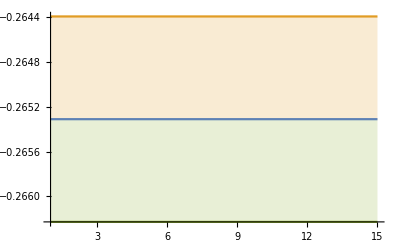

```mathematica
Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,15},Filling->{3->{1},2->{1}}]
```

```mathematica
SpoilHWFLOPlotN3=Show[Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,Length[meanErr2[[4]]]},Filling->{3->{1},2->{1}},PlotRange->{-.5,0}],ListPlot[{Table[{τSteps[[1,i]],meanErr2[[1,i]]},{i,1,Length[meanErr2[[1]]]}],Table[{τSteps[[2,i]],meanErr2[[2,i]]},{i,1,Length[meanErr2[[2]]]}],Table[{τSteps[[3,i]],meanErr2[[3,i]]},{i,1,Length[meanErr2[[3]]]}],Table[{τSteps[[4,i]],meanErr2[[4,i]]},{i,1,Length[meanErr2[[4]]]}],Table[{τSteps[[5,i]],meanErr2[[5,i]]},{i,1,Length[meanErr2[[5]]]}]},PlotRange->{-.03,-0.005},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]],markerlist[[4]],markerlist[[5]]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]},PlotStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau_{\\text{steps}}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3(\\text{NLO})",Magnification->1.2]]
```

-Graphics-

#### QCD mNLO - gauss

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={380,380,380,380,380};
NWalkers=200;
Nf4α1LoopBig={0.4,0.4,0.4,0.4,0.4};
aList={1,2,3,4,5};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
csvData=Table[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"],{xx,1,Length[aList]}]
```

({mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.7003175280298608, -0.9790622844247566, -0.6543366159771358, -0.5066068923558517, -0.5373748894788876, -0.8385854348462162, -0.5901716557624481, -0.43187548473161413, -0.8630653603801822, -0.4238633127507133, -0.6430817053345808, -0.6180792158986618, -0.38633121914403024, -0.3970951329445958, -0.3914493791146048, -0.45566846561137403, -0.593854595070538, -4.183585575949163, -0.7981885838752047, -0.63161061968833, -0.584553421654222, -0.45359382744901106, -0.379159295348036, -0.3431172779725197, -0.492772026508729, -0.36048501085916307, -0.3965789893970858, -0.4865709597482585, -0.5692704649341832, -0.4738452967412824, -0.3535158652203867, -0.31113572064134787, -0.27183749645522765, -0.26204081993039724, -0.28622818763549407, -0.2946988430047159, -0.31619789238328827, -0.28649869956847085, -0.2719038731488633, -0.2923147921250551, -0.28702798362704324, -0.2726012488673254, -0.27736467217429045, -0.30018052494359443, -0.32760665235737285, -0.3274143437741878, -0.3600484789598449, -0.31653198054663184, -0.3277875035586964, -0.30447741971037223, -0.29578207488231684, -0.29103959265250673, -0.3258162142944707, -0.36570845533887003, -0.3554004119347173, -0.34578433979198486, -0.3311721431422871, -0.33650288557926417, -0.3525555153140661, -0.34426174197102605, -0.37962407730022363, -0.34286953710155954, -0.32385466433004323, -0.3170610294200738, -0.2990698350682043, -0.2989897691662211, -0.42965013453037715, -0.3700629938905555, -0.4145073743865249, -0.4845911989092828, -0.5986053562277355, -0.3980733298135653, -0.3730997730957204, -0.32573360715644506, -0.278462021885511, -0.29126316464396623, -0.3142897397824621, -0.30043695934297765, -0.311172928698912, -0.2802054699215577, -0.2735589107104354, -0.2709256701210423, -0.2904045076790353, -0.28661320141293756, -0.2917419656598036, -0.2859568240421312, -0.2956450976972865, -0.298245853970108, -0.30030503162213473, -0.29678155362081526, -0.30069316942997876, -0.62752135267082, -0.3986273829292956, -0.35247285898170655, -0.4502018379833914, -0.3713101949311043, -0.3945022244830057, -0.3370038136177194, -0.3580641032032418, -0.39712224449429256, -0.33650160740316076, -0.2974279448941861, -0.3281766546380627, -0.32903706246949943, -0.392815337919972, -0.5136229895780965, -1.074765390573539, -0.3670513959955587, -0.4555574461679991, -0.3820105689891008, -0.5884694224740361, -0.5023577175537812, -0.46810989494474353, -0.3597922833897334, -0.31355164524685986, -0.2962302166032449, -0.32212957669836456, -0.33481482749859226, -0.31903906628951556, -0.30260531331509516, -0.2825646261643318, -0.27957450517809646, -0.2744484821735326, -0.26560021576708703, -0.2661790883717488, -0.26602869294994214, -0.26462404420166596, -0.29228635561259453, -0.2799852340255176, -0.29637208829161643, -0.26575077343915043, -0.24972750309622935, -0.24964282575741384, -0.2511056989986912, -0.2508652611654189, -0.2531404918240481, -0.25310951337018817, -0.25742517970287965, -0.24754299898139467, -0.2656572565027035, -0.2755304978220352, -0.3456648457599511, -0.30998116393908365, -0.3015200628335735, -0.27271691904520634, -0.29565550914285416, -0.31551855556452346, -0.2908944442964775, -0.29604680568881564, -0.3834069072844813, -0.34591866551976086, -0.3856911153830381, -0.3461869029440958, -0.31666508840085034, -0.32557726259336367, -0.3576044609087036, -0.3660543748678292, -0.3490446333942643, -0.3568114408666967, -0.3267166789897666, -0.31954028306975757, -0.31779999493870165, -0.32837551204818216, -0.31240814894124763, -0.3224690904081043, -0.38743622508077996, -0.3386322133396209, -0.29701440031907217, -0.29864856438962695, -0.2905720343167273, -0.2859595927871625, -0.2769112182462535, -0.2821761870841753, -0.27715754310148905, -0.27731642737289036, -0.2742960352982923, -0.2548851329746537, -0.2562590545635832, -0.26088584514688884, -0.26521750872797917, -0.25939358015657366, -0.2656678874812383, -0.2980923845689644, -0.2846407849754389, -0.2910481365917076, -0.320302932064995, -0.30763324036971174, -0.3061939468370683, -0.3087490989879395, -0.3212786542355025, -0.32446610006488735, -0.3056657829740838, -0.296547169448503, -0.3123070002189969, -0.3346085381500499, -0.3163278944593861, -0.3367822642608121, -0.3657878824925255, -0.4015587703014018, -0.4957059229784365, -0.3710716879973218, -0.5392255459270575, -0.5970065341849443, -0.6233340940921682, -0.4013312180528719, -0.40448827353537836, -0.41527672693861045, -0.4403084203511337, -0.37683945316394035, -0.4208617277006268, -0.4094983961931223, -0.37784112002533404, -0.5032032766912953, -0.357975293728302, -0.3827441608630254, -0.3689644596746115, -0.3932289091904938, -0.41674721698468703, -0.42498356080975747, -0.4367282069396866, -0.36583650292935227, -0.35661763351349324, -0.34383338344564046, -0.3313292869430798, -0.3478514761358084, -0.38405988052412315, -0.3685788509085092, -0.37053292548704075, -0.4322116553204234, -0.5192985218081565, -0.5018404821755682, -0.3916503113135519, -0.3490187203376792, -0.4251003517239345, -0.40855597633920804, -0.4127844005117279, -0.44138741991144853, -0.3661653572399253, -0.36570947880744853, -0.4063647664103218, -0.5405921513476544, -0.3993302974396264, -0.37244950848440384, -0.34664778233554766, -0.3756224888084515, -0.42248708684262287, -0.45482030572335963, -0.40593134786066315, -0.46776105154770475, -0.4578050978800896, -0.44094097870716076, -0.40548329315702974, -0.4845152621896971, -0.5661746349380892, -0.40405470868889126, -0.3993591772456492, -0.35260140264716494, -0.33193135801475626, -0.31663083678344967, -0.3395508463964217, -0.3360422641323367, -0.3109081658243276, -0.32553319353610083, -0.30675416694490204, -0.29193017751698563, -0.28060446260567734, -0.27782726415640685, -0.2788586966928916, -0.28585246904071276, -0.30887681382352383, -0.31262139755558377, -0.30749957655075233, -0.3102313300043655, -0.31110922267157887, -0.30353756066297355, -0.30377967318689797, -0.2872403508012288, -0.30116330298117255, -0.2945162917702966, -0.2895770981741841, -0.3029892241953118, -0.34242790699689957, -0.32750486920180005, -0.3934266624831875, -0.3206437206341348, -0.355165529840534, -0.38706339248311306, -0.35015722476562233, -0.3159998742354624, -0.2992435278356824, -0.28894458784057797, -0.29165023800631096, -0.2830795285292309, -0.31475169553733895, -0.3205495577767386, -0.314627075296498, -0.3085794517554615, -0.29581076195817047, -0.3093010181775975, -0.3249433862647445, -0.3227313512286295, -0.321396715793728, -0.3193756399521736, -0.3010922616460332, -0.2949640162331137, -0.29006072832551744, -0.2834112804026433, -0.28751278515408, -0.2829791882141136, -0.28294532436558734, -0.29474731061786985, -0.29850792332176956, -0.2877288976335826, -0.29107160712790936, -0.3016922310384439, -0.2966825679460057, -0.3071407821930073, -0.2982097638395412, -0.30524582815687346, -0.31138110794743284, -0.3878517828715493, -0.3084400847587674, -0.3115447926541738, -0.32299515451672495, -0.2987360218392012, -0.30271622533704334, -0.2959504472081523, -0.3018805786493621, -0.29280915276666303, -0.2862722765870037, -0.27612417370708653, -0.27860202707179543, -0.2738129531183411, -0.2884617445352364, -0.3003752850624243, -0.35025143284574806, -0.321040754771104, -0.290617694180246, -0.31216548895905916, -0.3433629707102377, -0.45448078672664094, -0.7324331527818491],[0.17228373153731974, 0.3140878348290094, 0.1425028957535653, 0.07596261602223726, 0.0913842231365403, 0.28706656849756107, 0.10762704154597354, 0.04587707525519381, 0.31032718872670606, 0.04462516206653359, 0.17126853530533495, 0.15544229701651646, 0.030979266839951156, 0.03718025413846918, 0.03487308783126524, 0.0598490474380428, 0.10769132230415182, 2.112070724586806, 0.22245516154949113, 0.11511119829061778, 0.09816650240095465, 0.05340452333284853, 0.023499600371089436, 0.04287398438485087, 0.05880960741356823, 0.024921487170198278, 0.02119465810178615, 0.06648592602719182, 0.12075331847506611, 0.06502376045744, 0.03776722170988795, 0.09943062462935748, 0.06169381303682185, 0.03663749581404842, 0.04596985522860986, 0.05122537349229624, 0.015612707796514167, 0.024576079860834526, 0.024196840449716088, 0.01902187235242667, 0.027449534619806683, 0.037511589545199196, 0.03746442968310757, 0.022158012679481656, 0.020573841200777418, 0.016628496102224548, 0.026887841395997116, 0.016679198741249977, 0.017800634373349715, 0.01194180130900044, 0.021824389113484347, 0.01668452169698156, 0.05832003255958606, 0.0862862474045772, 0.01693129929168575, 0.03886244926991176, 0.03384868527592687, 0.034829082342698096, 0.021647812057597714, 0.021165075140398844, 0.03473493780210576, 0.06619968849427403, 0.04952123199113023, 0.03819600693919507, 0.03372869236020544, 0.035542991747612655, 0.06421786795862969, 0.019537924008603862, 0.0501149018756349, 0.05809087226628113, 0.09294806953007066, 0.0509527950326669, 0.04358642688413088, 0.08319173775070879, 0.054802262515631375, 0.07833685767649098, 0.09697246897383592, 0.0596823630295678, 0.06435780932586276, 0.0488927812555378, 0.051534198673068465, 0.059594624433830734, 0.05838668454338129, 0.07067668278462802, 0.06617992931064501, 0.06872318279232867, 0.09154286289087518, 0.09152999164648018, 0.10576315112355336, 0.10116290578024895, 0.08550578279591457, 0.6451223729095868, 0.1748931838275661, 0.11094694942072562, 0.13905881750183788, 0.06553490644610128, 0.07421340360490668, 0.04613682230986739, 0.060992923851516105, 0.10177893466099697, 0.04195527679181821, 0.02706833512852699, 0.024797246144240753, 0.024540015806082564, 0.06538813348328186, 0.1655841945672726, 0.5184045158444011, 0.048059797034488844, 0.07846817266158744, 0.042856433036543407, 0.16011275642027203, 0.1033507041304595, 0.07185846192338896, 0.036433677444236895, 0.028667502760705562, 0.02125328315972917, 0.029443074051534304, 0.043538687250528736, 0.02991188483284592, 0.018669823978207867, 0.024925166283828102, 0.03312871428896171, 0.036814412532312074, 0.039144234328308, 0.03469108486744103, 0.03466693800680793, 0.03705315765253558, 0.11223767591282713, 0.06432675011248781, 0.09640066242713764, 0.045431540902615156, 0.027649049153125823, 0.034916257868332405, 0.031411317152053635, 0.03200369056941209, 0.038218226819094266, 0.04126485451362917, 0.04441220433401345, 0.039151739006363644, 0.06813845483542834, 0.08492615909945196, 0.20307507538011024, 0.11554652326432147, 0.0962096502452111, 0.06986799098528244, 0.09488560877712161, 0.11156013945256474, 0.06779102136639019, 0.07570544204064325, 0.16823577104015722, 0.10886853735142535, 0.13340322913904826, 0.09217035221827577, 0.06897969245036001, 0.07277584647320107, 0.07938217578449816, 0.08558138193567857, 0.08954241546926586, 0.10135119264555027, 0.08149901989036373, 0.05817345948360405, 0.07261418070846647, 0.06965711767849339, 0.06473737294200586, 0.06875140799672201, 0.13246993762188014, 0.08420707270316383, 0.04373800262635849, 0.025141270527885375, 0.019686708417326504, 0.020720306454297118, 0.019949301240239536, 0.024780724185890703, 0.016356412108266084, 0.019067698978018865, 0.019057373485734674, 0.017128287232557125, 0.019841112762358063, 0.020152188370858106, 0.021543978532070112, 0.019019202708360744, 0.020228626246279382, 0.04967871883201782, 0.027019538528380942, 0.02813818687595277, 0.04259345070146256, 0.035006397278127654, 0.03246918056829284, 0.028456979076966822, 0.027502885756535537, 0.035330271403487455, 0.02364751753851462, 0.01746672325413533, 0.024053009140794515, 0.023123414499766674, 0.020045909555021838, 0.0322171217987119, 0.07340213116935546, 0.10443987926510592, 0.17987291178482248, 0.0622414920831207, 0.18848745500175088, 0.2190568702683269, 0.22208484415487598, 0.06489260394447342, 0.05162870945191767, 0.04492775815460916, 0.044764548259092596, 0.022909050353419967, 0.06041604388674777, 0.03592590281723135, 0.04329147238640128, 0.11275256047472894, 0.03162215514771199, 0.05174727716441982, 0.0279559511827656, 0.032839923078664755, 0.06513998720437189, 0.04659568804705546, 0.04500539010442736, 0.022421250596617346, 0.019309345738277982, 0.01698070419381494, 0.017148735209416375, 0.02024739347104453, 0.038373241361239784, 0.02930508738035051, 0.025456068877237142, 0.07583184991104222, 0.09775990515067258, 0.10573684564517813, 0.035670267456278916, 0.03735306772654287, 0.11783154835503051, 0.09642839903536121, 0.07985110610488427, 0.0899936672504892, 0.04293341540539285, 0.03865567761342051, 0.06186504089928383, 0.3121457337738649, 0.05935151433641152, 0.04033568318082653, 0.0342375282214961, 0.0416506580152643, 0.06303178058791245, 0.06941664170276059, 0.038104811564681075, 0.08184079190523848, 0.05840930011780051, 0.05399343137208781, 0.036036167014804915, 0.05743684193583818, 0.09123721532486373, 0.02038975706904339, 0.02999088605831539, 0.021104049576728606, 0.022337337909925, 0.018199254149055558, 0.02214015272524606, 0.025441951879493194, 0.024776248339935317, 0.03674073979374953, 0.012428688572707241, 0.01315973032667513, 0.01764212133793969, 0.0127099072181514, 0.02634506891116535, 0.02709508787270895, 0.04080160022195656, 0.04362340997037626, 0.022665755902878833, 0.03469734034643543, 0.03954715699864526, 0.0324597438359151, 0.03911490582540591, 0.028180498350676292, 0.041535997656095995, 0.0281426049118164, 0.023782918142190048, 0.019226265978051695, 0.021549191734600005, 0.027711259373316602, 0.12025403524266222, 0.05164637436373161, 0.08382376162244416, 0.11795859632242267, 0.06773848826550093, 0.031081606408628108, 0.024241561715040816, 0.025163843489820356, 0.01690708124050887, 0.014280536642469564, 0.01885937776692952, 0.034829572768749414, 0.03551961523610698, 0.03443644280097509, 0.023476712841389417, 0.033488716083564844, 0.04277533383134473, 0.03796207147022902, 0.04396658326888837, 0.047022204770311785, 0.03528800804762314, 0.033154057393766714, 0.028384628514832446, 0.025740038629457552, 0.026643847692075274, 0.022832606471166493, 0.021925164842110708, 0.026162724207835067, 0.028188555369078747, 0.01950876095522896, 0.02146728197594706, 0.024948904284416387, 0.01932935736073133, 0.025849545804212514, 0.02675675500897865, 0.02822760233666787, 0.03901365039866982, 0.11851738428858273, 0.033791960677783076, 0.03702950295070555, 0.04645462171465261, 0.02858544258258191, 0.029874496016343025, 0.021797058433503713, 0.02242195726145635, 0.01794405229605247, 0.013687718731290438, 0.013311348801679921, 0.01511383905958543, 0.011577285296661221, 0.021432892871431835, 0.02825783169869241, 0.07383671291727693, 0.032217566725785456, 0.014789686772245505, 0.03165278376002298, 0.0330249545050397, 0.09894569806584011, 0.23217139227101968],-0.326558,0.00176751,1.10627}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.23944334551512916, -0.24863142024924217, -0.24744842191680685, -0.2590652284314573, -0.25337785136006596, -0.25952762646846367, -0.26837755688346676, -0.2652123353419356, -0.25632926221211505, -0.25975257389326395, -0.2534386266550979, -0.2529314535383581, -0.2502321217697368, -0.2489125961276981, -0.24648222171172837, -0.25439100222802025, -0.28793456037876264, -0.30778041283931545, -0.282808667073596, -0.2768622119419269, -0.2799099288200245, -0.28469666279521116, -0.2676815593743011, -0.28691530023070855, -0.2777602782696912, -0.28298650765654515, -0.31492195347522023, -0.3021684475838165, -0.3247564155875484, -0.3391172528299109, -0.35966163791769756, -0.3181147646498943, -0.3294126837924702, -0.3742819827574706, -0.3203760769805069, -0.2913760690484057, -0.30865323535276257, -0.5406868785695341, -0.4555563416496878, -0.3817719372567775, -0.59334640670898, -0.38724658926817696, -0.42573079205936804, -0.35810659693162517, -0.3438187657319201, -0.31644337618257135, -0.30194382122727287, -0.3020608566295416, -0.31524682993928593, -0.30276625446589245, -0.3031707735097885, -0.3040293196879714, -0.2865537630442822, -0.2798560110600802, -0.2851905853232861, -0.2879618825225022, -0.29569735921008117, -0.31513729169542043, -0.31011249159741733, -0.31689468652730435, -0.32479718834417115, -0.367643342275719, -0.3335288102601179, -0.2991944466677159, -0.28555099876111195, -0.2925395119423305, -0.2761202152825832, -0.2738957955299014, -0.26898329764434853, -0.27336208578254295, -0.2764073525581964, -0.2624946758212225, -0.2723842743180954, -0.28296137066983335, -0.32302160566350696, -0.2775637970078149, -0.28080842000052236, -0.2686858096585341, -0.2615266886810298, -0.2581889398894343, -0.24708911890104276, -0.24389836912365354, -0.2516024848952432, -0.2443418438199303, -0.23883073040854386, -0.24099914070905082, -0.24025345559147016, -0.24965048115366137, -0.24727047501362515, -0.250766891660115, -0.2450532368788661, -0.2576186834021845, -0.2496429506445328, -0.252872679539496, -0.2432697029262575, -0.24551142331975243, -0.24746349727003245, -0.25450865158327396, -0.2535608768473849, -0.25727016189413726, -0.25368131797697985, -0.25990266344622104, -0.2595274268271407, -0.25469308527886303, -0.23905754954982114, -0.23880646057604765, -0.238617487220662, -0.236345718860902, -0.23307877653806466, -0.23092533613026275, -0.22423743637040544, -0.22667163064718232, -0.22823574189722204, -0.22012857063349878, -0.21854235786049475, -0.22195207469635897, -0.23248893167637824, -0.22842709545428974, -0.2158673724611696, -0.20473363570504083, -0.20379685464912864, -0.19986748916255626, -0.20089396009092358, -0.2039825659824582, -0.20347415251253642, -0.20958397273984355, -0.20688863154145515, -0.21160491212134216, -0.21254808007683315, -0.2122328587666462, -0.21206948175411933, -0.21716590534582741, -0.2167884527268506, -0.21352585430789756, -0.21473430798018717, -0.23043893119173012, -0.2362292531003238, -0.23530320033561794, -0.22999169510912978, -0.22980993647639886, -0.234034191673466, -0.23863852240133315, -0.23678110414086292, -0.23342262760132068, -0.23974744528436784, -0.2486303340496639, -0.2325793297057207, -0.23062150791374714, -0.22907422343786032, -0.22797089589934766, -0.23560786666307623, -0.23918041882236418, -0.23368616373651185, -0.2458015638315937, -0.236794473434187, -0.21948238041110993, -0.22121245254961067, -0.22306206609805268, -0.22994156483020062, -0.22890234691984448, -0.23262856689942085, -0.2424848364319972, -0.257191608660814, -0.2593681778367007, -0.24525494685719548, -0.25809794395173186, -0.2579580794734932, -0.2438896329717417, -0.24368909281092846, -0.2627469468401887, -0.25044002160853823, -0.2527824209009448, -0.2698600589984013, -0.25875716318533093, -0.257488140462615, -0.25360249913538463, -0.25722808713501927, -0.2502662338511671, -0.26737623966337104, -0.29001505197832006, -0.27995806893810615, -0.27220685069206035, -0.2797973888160756, -0.2862899748830439, -0.3007707229552557, -0.2907004446380112, -0.2911470480638603, -0.2828311009662162, -0.27550350213750674, -0.2895447929135538, -0.2567762441552288, -0.24394987736734683, -0.27370257781842516, -0.4350251361198999, -0.33394725693074706, -0.32668007406443994, -0.3490780163145076, -0.37916000486994983, -0.3302355192344895, -0.29343241555556393, -0.27633896152792153, -0.3131747842016239, -0.29918895472866835, -0.2825308206230378, -0.24557956202005035, -0.2540969800601518, -0.2430006118255158, -0.26939336795438285, -0.2746146677782595, -0.28446458628042903, -0.29450422282143973, -0.2669881338051599, -0.28580861490769083, -0.2946935796934477, -0.28856231925999737, -0.2769087389492398, -0.295742339781558, -0.28145572030710314, -0.2849089635572252, -0.29208699012192063, -0.2886612169301709, -0.33039477187958727, -0.3474658639927851, -0.3420790582016609, -0.35243159208074487, -0.2848282798012783, -0.27885391687010264, -0.29202294605738305, -0.2958041153643049, -0.30650546718091204, -0.31204829789562527, -0.30829500718127945, -0.30861702848618433, -0.3484918097696769, -0.31563345516343766, -0.32640019244250823, -0.45125783290099764, -0.3919359462042623, -0.4384193432688052, -0.5080415374818554, -0.4966920060211853, -0.37690393755554735, -0.3287914737449586, -0.3221671558362288, -0.32887974447700363, -0.372239757363612, -0.3573363366831731, -0.3356457886422951, -0.3155347288177123, -0.3026506647530234, -0.29357248487709975, -0.2888597679225105, -0.2857432558846727, -0.2852608207614667, -0.2952124025843357, -0.26960125417091896, -0.2737958200371316, -0.2552586499237569, -0.2513382936770871, -0.28805405674082263, -0.27761563633501124, -0.26338577906622324, -0.2878304004132861, -0.3039794657638544, -0.30417947116779276, -0.34445871735338496, -0.34434964149205455, -0.34688917518665835, -0.3536967481236027, -0.368191480630478, -0.3487665466544908, -0.3462504956362808, -0.35394634547888004, -0.38763787724038506, -0.3341611457505786, -0.36468467650480424, -0.3278467044813609, -0.3560857021944724, -0.3105068927601211, -0.32379649008816486, -0.3299205038910283, -0.3508544370919934, -0.3566227065132508, -0.37458704637008494, -0.29934488949454896, -0.3181605647928674, -0.3886889967661256, -0.4249752252949912, -0.4092004822812692, -0.3652182031363906, -0.3380268129324819, -0.3278470531134437, -0.3025928244022079, -0.3222972139730541, -0.3224954575760937, -0.3117791857098907, -0.2890760547523799, -0.28492882332138564, -0.3030095439310686, -0.3130437393196353, -0.31286368307950635, -0.29173160252196795, -0.30508559222630005, -0.31247509186067385, -0.3251868658744797, -0.28823915804973027, -0.28657714640794174, -0.30588066695458666, -0.2575073839785953, -0.2393051799957729, -0.23383355215312016, -0.24216228152705546, -0.2261544478935031, -0.23041583299325358, -0.24436344453960002, -0.2431780442251717, -0.24575781383373713, -0.22493981569012034, -0.22818745157406523, -0.24822802636047525, -0.25214574184351357, -0.2950452761769331, -0.3234033225360683, -0.33641148568361096, -0.28451874378850994, -0.2609423186450677, -0.22924337702844405, -0.2281924451710288, -0.21015285631333216, -0.2042922350535824, -0.20812633151610718, -0.2150633017329288, -0.21259691382030074, -0.20775871899395532, -0.21519824798735576, -0.21270612595176783, -0.21213255990217092, -0.22181511399149278, -0.2170117429768324, -0.23371178651785593, -0.22759269989228237, -0.24815034870111696],[0.018978307265810852, 0.02536307944330167, 0.026430631888177434, 0.03076993950913641, 0.026584886813086905, 0.029447118825771123, 0.03270441977479485, 0.02734268848365602, 0.022590291337062012, 0.026016295113083548, 0.018677939046613138, 0.020516021819446333, 0.02079853383511955, 0.018823278490147803, 0.015209971833336049, 0.01828725283655579, 0.030074255331808478, 0.03960341589125768, 0.031973689664692, 0.02819680679853673, 0.029277693684560836, 0.033014014624082044, 0.023640323425545926, 0.032688143421937293, 0.022598804165898607, 0.020351084245919727, 0.03324331765030118, 0.027574944623674175, 0.037460025045890986, 0.04315091723521267, 0.05900508936619161, 0.025158708221906988, 0.042386578995927814, 0.07368473727446957, 0.0360400480905022, 0.023830328851501808, 0.026821100816615078, 0.23262337441175363, 0.11456791675020532, 0.056505004849385115, 0.2275269792177128, 0.05086390551911848, 0.1298396030901342, 0.05828420349247254, 0.05098078869422584, 0.0354048486185085, 0.023718677587553152, 0.021163699602816912, 0.029834639368283206, 0.027797274851234344, 0.031034499916776415, 0.04379100408494708, 0.03219027833192835, 0.028307770312368058, 0.030304564739163854, 0.040503517209561433, 0.049763848455769706, 0.06418359698996397, 0.059175629999646824, 0.05979612814173426, 0.05754136520757104, 0.06663638221877943, 0.04439423861911208, 0.028773417986811094, 0.029136635333493838, 0.027977896368075527, 0.023427314219245106, 0.02553026333954009, 0.027103096578026103, 0.030014336431956893, 0.029131363801745903, 0.019342053209502073, 0.025861496868669776, 0.02655500440434204, 0.058667075197883646, 0.02538198795329026, 0.02916283915453109, 0.019410018920470166, 0.017473567391123216, 0.01723716378021285, 0.014822391399729764, 0.016334385775134845, 0.01859731048114559, 0.01457654647020549, 0.01339741340690008, 0.013465046288737261, 0.016493546408135436, 0.016814631403651147, 0.016113039874162804, 0.018096290392244307, 0.016836215468924998, 0.021258323213154313, 0.01874411027876465, 0.017565726470400864, 0.013680274016375824, 0.016382077498941366, 0.016369603096970678, 0.023421806120896664, 0.019668391556284286, 0.019270013856731667, 0.018504741478650617, 0.023158994807690035, 0.026914870350652743, 0.024197912743298994, 0.015518224522156652, 0.013802811359307172, 0.013591852958413813, 0.012504050568019986, 0.012104492832202267, 0.008564749519470565, 0.007331842462741189, 0.008130822498480062, 0.010941395698050147, 0.011455063435508683, 0.012449186074748394, 0.013733894716364398, 0.02142588104018606, 0.020578185186687324, 0.014057501052518752, 0.010774387351908585, 0.010850285619350055, 0.008321743831598394, 0.009088660221930101, 0.009306258426144923, 0.009986731206107683, 0.012519202205913202, 0.011381881755811942, 0.014251954628137636, 0.014167523025873619, 0.011278573507757116, 0.011062090437774699, 0.011156823736917136, 0.011445427060843746, 0.011793452404102749, 0.012533093719872976, 0.020703116502420252, 0.02669239177757646, 0.028768397929031356, 0.022038767978607213, 0.01745029891984613, 0.019094201995416112, 0.019226227502806666, 0.01821095243368242, 0.01567516985700842, 0.016244127781583368, 0.02020914890156591, 0.011039176946386767, 0.011265871694856395, 0.010060986935594011, 0.011873635654192666, 0.013814638383683171, 0.015556705181502912, 0.015476742862771857, 0.02038169925399454, 0.014908530709234374, 0.010661549132435198, 0.012194262147086181, 0.013479760940631033, 0.015647900332567254, 0.016496175369350476, 0.018076590855056418, 0.021868995028380325, 0.025272873397833937, 0.026302808191993054, 0.019101601648107737, 0.02483179333690214, 0.022219534751347043, 0.0187973342146702, 0.013651859641498494, 0.025959361304413394, 0.017453320810786693, 0.020413440329832312, 0.02676506194954201, 0.01961248856021475, 0.02225466854411882, 0.021918042815884123, 0.019402335865028892, 0.015079925014330508, 0.021134617495610672, 0.03527844479925193, 0.030011042451209717, 0.02862274542313395, 0.03853641009394214, 0.038744749999964904, 0.03786396351021011, 0.03426862666168696, 0.03674731983573014, 0.028765482426038498, 0.026097335301393403, 0.03374586204188925, 0.017424203949888462, 0.015529266338981834, 0.0305403642390475, 0.25391591386707774, 0.09284166844466803, 0.04507085451475748, 0.05606329623893257, 0.07088904324135585, 0.04418936349534035, 0.028919989685140587, 0.026103290236871725, 0.04694951370100117, 0.03857202271803055, 0.03409001482225357, 0.01648204830948563, 0.032375878031608775, 0.02005177435808094, 0.0277004604282119, 0.026884953845105357, 0.029248717061480307, 0.03613601873619822, 0.025797943328579435, 0.028953879502701913, 0.03553049381456746, 0.03148706257466052, 0.023098050214964246, 0.03153187728162281, 0.028784382482304846, 0.02570331993703188, 0.02729019304410376, 0.027984841678258453, 0.04554819513544835, 0.06060321953610268, 0.061934545122176964, 0.06567804196789927, 0.028682789171325208, 0.044465874076410145, 0.05103480070443179, 0.039890844819904646, 0.043139709052214203, 0.034205490241115695, 0.042367237890417145, 0.04460609959099181, 0.042848513191617275, 0.031295934191278886, 0.04996654717991867, 0.16760704836888723, 0.08697033943620568, 0.0717841527755413, 0.10968992379012815, 0.11028022021231348, 0.05353745278103759, 0.05095415615836604, 0.0469340977169912, 0.05161564493977281, 0.07060267383898382, 0.05824444106921342, 0.041098555720649084, 0.03327888254847926, 0.022107583346287193, 0.024522909814600882, 0.025189595888695647, 0.02269526596472128, 0.025194391674411298, 0.030668902872019673, 0.027820693353297222, 0.03544783329180655, 0.027127020296269556, 0.03447709497167802, 0.06434267820416513, 0.05608508635914078, 0.04802584829152807, 0.07023733478328888, 0.07596977061680456, 0.08396497110333226, 0.1173903679855259, 0.11579867948279589, 0.11117585313848305, 0.10469596168130164, 0.11261397303019828, 0.0845548220338841, 0.07996887070626274, 0.07662169753454905, 0.09260319130530455, 0.062283871061041385, 0.0905949682802875, 0.06040443927801875, 0.08758802676832225, 0.05904428372302764, 0.056479090645698664, 0.051776428974524794, 0.05170339501533602, 0.07244638840370476, 0.08009354032279399, 0.04243464024883743, 0.06062546166606716, 0.10996511832570283, 0.13507621719788565, 0.127939518636405, 0.10309328283922356, 0.08533649217580495, 0.08157839993870464, 0.06673112446728939, 0.07443394587306351, 0.07694356048705321, 0.0697264703485133, 0.05742871327201412, 0.05779805331964503, 0.06383677865371527, 0.06711096105286932, 0.06413095766880143, 0.05078091693836859, 0.06314477894026027, 0.06495607607228256, 0.07410215206421918, 0.05471091971793001, 0.05335056842586268, 0.06545040184393755, 0.04152498300448961, 0.03214199243669771, 0.031273295343126825, 0.03613846554338758, 0.026878052039757388, 0.029231054979263208, 0.03318666829002428, 0.03127858062388008, 0.026886163695763708, 0.014403626164665305, 0.013300404529586229, 0.020366058669207862, 0.02162537779404345, 0.04104539680914274, 0.05595121403451622, 0.06514520192155472, 0.04100113455631784, 0.029202430029227667, 0.016230402582269744, 0.01231627552101739, 0.007964917525241366, 0.008766984137019422, 0.009095273041680528, 0.009017176048873251, 0.011616956118372499, 0.018063009164814434, 0.02871273983289279, 0.030295130187538197, 0.022475186374341382, 0.022264257015347778, 0.016690039734555035, 0.016441414617438314, 0.016674507837675212, 0.024382148428893097],-0.215305,0.00179714,0.625318}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.17095772831390232, -0.16927066685414846, -0.17022925105695746, -0.16591870724792773, -0.16890056928508845, -0.1720622069624345, -0.1727057261258174, -0.1748375705332854, -0.18425054443675626, -0.2013133666239361, -0.1884549386852992, -0.1910995143900018, -0.1977504589511562, -0.19441110560642946, -0.19983313711983797, -0.1961153886312395, -0.198999143524485, -0.20112472686189525, -0.21191562727598534, -0.22233877628877735, -0.19991084861212233, -0.1988573911527014, -0.1985560982086185, -0.20356394377090536, -0.19827442816498858, -0.19869285937511133, -0.20256361755558983, -0.2050879465742272, -0.2169633784793364, -0.2098921038530156, -0.20895957010820185, -0.19978950873020412, -0.19631221412712663, -0.20046524625371123, -0.20565917509881895, -0.2038084159742558, -0.21123461946801603, -0.216264481322352, -0.21656948001090243, -0.2240492243221009, -0.21933141103905768, -0.2214542522598363, -0.2148206627398742, -0.2176067274692166, -0.2264360042828309, -0.2366759265150305, -0.2237420265140886, -0.22634429155586203, -0.21160905056318272, -0.21516661873779058, -0.2111355977721984, -0.20467316480762715, -0.20344720366493305, -0.20601736350711647, -0.20812543911499085, -0.21066013404226933, -0.20834657625002426, -0.209396023918672, -0.21107900374494143, -0.21044431464090857, -0.20384302452334185, -0.21021194823649866, -0.21059905359352138, -0.2059156393303405, -0.20927250669879396, -0.20661136904741637, -0.20820510888264854, -0.20937928726450727, -0.20914687257986253, -0.2210064653465159, -0.23644771299686923, -0.2308079946709019, -0.23312051409147144, -0.21132127755972324, -0.2076782215335256, -0.2012728348374468, -0.21465742803717353, -0.2110423770049816, -0.20975542374678796, -0.20796201545626333, -0.19923418814661303, -0.2042606499066451, -0.20023566016675315, -0.19738359832834826, -0.19728354264970316, -0.19826422356071086, -0.19824087106923047, -0.19827097269539107, -0.1986210166343468, -0.20021611167347556, -0.20145511678488395, -0.20789535678382248, -0.20726109214005894, -0.21110814481729598, -0.2058052712851613, -0.20749901933870682, -0.2086293741550051, -0.21439337249852233, -0.21279152407394572, -0.21872375591059626, -0.22532187212461832, -0.20489011112709948, -0.20212693994753128, -0.20796878329729748, -0.20433176308291826, -0.2024849476160352, -0.20567428284825953, -0.20582459337550682, -0.20108002864830404, -0.21362922301224163, -0.20520823766958504, -0.2031109807417743, -0.20639361447038387, -0.19779134760535255, -0.1994366678845465, -0.1889665471951946, -0.18474207583291402, -0.18244463956760068, -0.18416319234471726, -0.17936310437208544, -0.17366784406934918, -0.1732193140788829, -0.17362745705864605, -0.1733607768459898, -0.17205404465783886, -0.17182589992216324, -0.17276395705376582, -0.16927289833021367, -0.16928001660856115, -0.1717048466984374, -0.1688346955655816, -0.16952267136466947, -0.16993815473316312, -0.17353786387122278, -0.17711674308919959, -0.17914533374222635, -0.17756706286577828, -0.17542052752505033, -0.17985634545433182, -0.1813968214565281, -0.18762312526417665, -0.18716008976280818, -0.18209323951046646, -0.18443848294078785, -0.1915706734237907, -0.1972062693404185, -0.19427145264490178, -0.19282675926988627, -0.19375653773629983, -0.19160188816756923, -0.1895815590558198, -0.18656362118695047, -0.1831638269423944, -0.18330474069992894, -0.18284265702129754, -0.1810549253018064, -0.18055788712851484, -0.177954583661788, -0.1787678084634343, -0.1772082456954973, -0.1766004830454726, -0.1784358124260682, -0.1819196960613916, -0.18255146336146416, -0.18609025369098042, -0.18627865390505602, -0.18780427417446927, -0.18327876435417542, -0.18314933038278733, -0.18311600096240604, -0.18464260327301735, -0.18400419281033717, -0.18952517658706594, -0.19012715914185263, -0.18416966431900889, -0.19112285574029045, -0.19176327449807046, -0.19356488330133978, -0.19162282473516654, -0.18480207401655113, -0.19040266977161519, -0.18326301605336148, -0.17835678413840272, -0.18053525329056958, -0.17822020598247218, -0.17863627609164862, -0.17540967293173423, -0.1763636568566961, -0.17616942031730526, -0.17471727507912488, -0.18024807723836983, -0.17698110762163438, -0.17594089008008193, -0.1741306994700021, -0.17702965438025162, -0.1829508329733235, -0.18054912724554656, -0.18368107847524257, -0.1810916994005365, -0.18266174897897625, -0.17932859874506163, -0.17982641650780176, -0.17941979033681987, -0.1758949151109387, -0.1759368832737038, -0.1749555269299251, -0.17430779826595952, -0.1755279941308693, -0.17647725742174206, -0.18030916574469666, -0.179284764593973, -0.1793182083316212, -0.1803187732284901, -0.18058489456893595, -0.18238444547437171, -0.18201111920724522, -0.18159882282053014, -0.1831966797199426, -0.1868409783711397, -0.18848344573871373, -0.18830049067029914, -0.18741893179941282, -0.1874111342899906, -0.19196697952644187, -0.19244177294561945, -0.1948078556778209, -0.19142853933919715, -0.19771740048072936, -0.20737657104820598, -0.21271602253659216, -0.21150703714036873, -0.2091526801937284, -0.20605628107553706, -0.21089336630795272, -0.20879532686792582, -0.20582243290675162, -0.20345783754449495, -0.20513244107458334, -0.20567137498891583, -0.21434742905721932, -0.21376008775884883, -0.21080372320816945, -0.2066993359583604, -0.20702404368325736, -0.21611951901857498, -0.20686809547802762, -0.20410210081864097, -0.20989026702710925, -0.20919932186714435, -0.2175011567742971, -0.21122678343793433, -0.20735318643727588, -0.2055077847106884, -0.2078038002218157, -0.21084158287098131, -0.2064724197700015, -0.24606195759984953, -0.22619528401909117, -0.21905302707294635, -0.21245254235370117, -0.2142303638331325, -0.2275009763635079, -0.23948174618318685, -0.22419268815500837, -0.2438465706881627, -0.23405530801455482, -0.24075236708895756, -0.25887159432316365, -0.2480902796050707, -0.24319499248910423, -0.26135804300627014, -0.2505059430032843, -0.23628617152464443, -0.24631027551455772, -0.25681285863965714, -0.2417239320161467, -0.23383953308599983, -0.23299644005649797, -0.23707518141482592, -0.23788543440410567, -0.23716709354616583, -0.23712644330627844, -0.22953993143428006, -0.22846991017329726, -0.22977536245563343, -0.2311423278362503, -0.23324206827439753, -0.2345035561948154, -0.23649349002644723, -0.23156857637007253, -0.24604283905906082, -0.24280698434144007, -0.2581283095565214, -0.25640699576194675, -0.26952807974007825, -0.26149926569995957, -0.26859139276546773, -0.2850447342740923, -0.3048238317793947, -0.31596186619676997, -0.32680552029386595, -0.30322301250213723, -0.3234580829696132, -0.3422802899817467, -0.3315548944942206, -0.49962797434578615, -0.3432214411898745, -0.33843489993968695, -0.3394528107321946, -0.4861442941194352, -0.27825847788016866, -0.2760292913745429, -0.27331903049300355, -0.26806826846943116, -0.26828083444232576, -0.2706284368175238, -0.2662156916003856, -0.27187768076612046, -0.275763732443517, -0.2849898307306097, -0.2957855290897993, -0.2943220211037533, -0.32411997705238865, -0.29995082042703636, -0.29503240218875226, -0.29439183639749145, -0.2730568433777322, -0.25292658507510224, -0.24346244308945042, -0.24572079721631943, -0.25104398537986317, -0.25068062397112945, -0.24851211746115093, -0.26069914594321975, -0.26242774952122205, -0.2965831123833864, -0.2735429427307705, -0.2645992624371251, -0.2606904712370569, -0.26979810631280493, -0.26133239033231564, -0.2587049410680912],[0.011552578291338617, 0.011018689641071737, 0.010846490487846507, 0.009141540315279528, 0.010646193003920133, 0.01189054072808037, 0.011779052359462517, 0.012803616633126236, 0.01796220383372296, 0.028382155259890487, 0.019534488918959512, 0.01997135020121168, 0.024114163824855754, 0.02198412520808004, 0.024797677722184303, 0.02134186682740002, 0.02173288786214326, 0.023184394968641657, 0.030013424272422404, 0.04007975806694925, 0.021055096266249858, 0.019880163314709185, 0.01942311366078895, 0.02096364136520224, 0.01840271612765387, 0.01748588743217091, 0.018241563422194757, 0.016899683442164266, 0.020243947489502853, 0.01823964878565225, 0.017494629077591042, 0.014922830221783229, 0.01412773327774374, 0.015732347989550588, 0.018119011096316286, 0.017465641307392744, 0.02014325877139948, 0.02208182212495348, 0.021262408818923193, 0.023532916475745628, 0.021967578064521626, 0.022622785903509444, 0.01970529405678854, 0.02111243427729618, 0.02260086775686576, 0.02894264635730074, 0.021075557355064934, 0.020986070771679452, 0.01704453034783742, 0.019046303891056375, 0.018695912304349714, 0.0162595386086263, 0.01738744299361346, 0.01867292195788879, 0.01953397757946419, 0.02148473010358459, 0.021154567619158925, 0.02019469175605712, 0.020052542548502382, 0.018255598318467698, 0.013954282340408564, 0.015259352633185608, 0.014106443571202026, 0.012796214353485524, 0.014803502996714119, 0.014008222324235571, 0.013787178479578468, 0.013923248399013613, 0.014123044452275208, 0.018471171841436727, 0.025481335716932327, 0.026296907445957203, 0.029547361164860272, 0.014429638191306961, 0.012481793954461499, 0.010672465407873102, 0.017075688471566333, 0.015813281275759802, 0.013489850456005058, 0.013601077600641302, 0.010555090232423328, 0.010759289848917707, 0.008661349715270467, 0.008064189508805388, 0.008135121640958183, 0.00846923327058389, 0.010357406562921263, 0.009307042550523732, 0.009647853302118042, 0.010789166063214645, 0.012882481121360492, 0.015647732666840077, 0.013619384264635858, 0.013610975332382792, 0.01092684750125752, 0.012929786635817031, 0.011844542022914899, 0.014976333603375391, 0.013432281085615854, 0.014400787600012399, 0.019860624916222744, 0.008820675678657349, 0.008134280382486791, 0.010879115518023688, 0.011003892686410414, 0.009620721257760478, 0.01155258482702608, 0.011074700433469547, 0.008538384787098665, 0.01408685085592504, 0.010727462533301941, 0.008901981954811112, 0.011294021029150574, 0.009194022929723315, 0.013152721436091334, 0.007217112447343613, 0.006870360723041643, 0.007516093332555891, 0.008343673884336425, 0.006776608458405379, 0.0042405090651188885, 0.004686131868844653, 0.005505068065458062, 0.004576966590948541, 0.004908077672862259, 0.004442536870815562, 0.00623250605734112, 0.005534738332955587, 0.005350024374015757, 0.005130940241586489, 0.005066673803863432, 0.004895753062400337, 0.005011909716515321, 0.006721437426258537, 0.008340077056143045, 0.006952506461886589, 0.0063638432077287345, 0.006257384373900912, 0.009152070296485772, 0.008313782342649038, 0.010757064780038078, 0.008431444146684222, 0.00720030058948741, 0.00823430892325451, 0.009369298576080926, 0.014904929555122575, 0.01312661055733876, 0.012399110279175904, 0.012262209107311944, 0.010851825796694385, 0.009435788732337793, 0.009046747860298722, 0.008178232668101528, 0.008125221721616534, 0.0067477785201683575, 0.007141462328196637, 0.007865382491649505, 0.006701121090414889, 0.006705264957312365, 0.006677388333545285, 0.006481511283348185, 0.007102801546408915, 0.007745003195675518, 0.00813875946183983, 0.008944227117187564, 0.008594564093383206, 0.009059814048915362, 0.008967142073044684, 0.008822256878131712, 0.009020775345219952, 0.010892982133677388, 0.009965183163145866, 0.014401616394205416, 0.014540712712868031, 0.010536811597011584, 0.015502547586465574, 0.015900244038217066, 0.018975041678929196, 0.020540107746206928, 0.01516425531705984, 0.019840582373255585, 0.012764426197707004, 0.008890802900898383, 0.01171946628930587, 0.010067983848641273, 0.010011859717179043, 0.008742939730194656, 0.009805195856770518, 0.008876538051761959, 0.008547907491114526, 0.012110111021667112, 0.011127994326789816, 0.01108429614914799, 0.00918903823956185, 0.009984302697472866, 0.011864405140490225, 0.010363323772778193, 0.011756476491800146, 0.010528235658026899, 0.011033990158645039, 0.00957334573196464, 0.008775015906197269, 0.007624265209282543, 0.007074225999364373, 0.007251820447993835, 0.007703898123303044, 0.006922168976328675, 0.0072006191068111555, 0.008616193856597315, 0.009216575616696367, 0.009737997182290372, 0.0087988634189284, 0.008919281391777794, 0.008410627586668763, 0.00817605729107103, 0.007535588932957983, 0.006920442142171853, 0.006725206965818101, 0.0076801313222699214, 0.007861129889041472, 0.007455801960092219, 0.008007251001421065, 0.007730463324004313, 0.009003486069093566, 0.008873098475495115, 0.010026345797952045, 0.008433984584757678, 0.010383781854093449, 0.013649139938469328, 0.01896200575362877, 0.01906062224042415, 0.015909845110855487, 0.015128367676500196, 0.01619179225814987, 0.017047215555903637, 0.016515307980285873, 0.01437877624079365, 0.013926232292105234, 0.013140840687421874, 0.01654627167716581, 0.01503766727704639, 0.01473874752305418, 0.012528709317140322, 0.011536351920942049, 0.015083747089699768, 0.011233294969903865, 0.010595264186851852, 0.011314354812147135, 0.012092400170753503, 0.0169201172763409, 0.013524653401954266, 0.015350056506626285, 0.014425899653932891, 0.017237279444752732, 0.021760943032147775, 0.01934193658890566, 0.0639441158632155, 0.03354402917814295, 0.025997374205600273, 0.019176171394485794, 0.02235228782367108, 0.03150679889878476, 0.03782363181969503, 0.025172610762635397, 0.034481890950075984, 0.028473945544920342, 0.032269763254007856, 0.0443463008849456, 0.03865186239230883, 0.03855360299326249, 0.047745699978431824, 0.03596884060933184, 0.026555318931063346, 0.02846705409228618, 0.03598893744477935, 0.025707902613284733, 0.022421680372649293, 0.02008153827132119, 0.019691446438773946, 0.02234037587846403, 0.022701657076077457, 0.02351867831316503, 0.021100554408061845, 0.020502650329506093, 0.0215723097370985, 0.01828741581184428, 0.022630516047102905, 0.021765644493393094, 0.02220818447375193, 0.020115796732939027, 0.023640315664771844, 0.02571091520992068, 0.03142859654951347, 0.03463182903575251, 0.04800747697788778, 0.04308146569475115, 0.042092497571296836, 0.046241377371232614, 0.05906194737067495, 0.05897316543957436, 0.06227760266153402, 0.05707657719689921, 0.07146784852660258, 0.08039356549432641, 0.07481638437576262, 0.2442577654785382, 0.0770951282860412, 0.07529158141731222, 0.07491432910093845, 0.25473608286902194, 0.0374420508017923, 0.03287235970705791, 0.03035144343981163, 0.030759707338638056, 0.03124653198061375, 0.03074664167620761, 0.026833978286561685, 0.024809330946463877, 0.025019535455081204, 0.03488883428601249, 0.04581639417939349, 0.04887356390975315, 0.07074909171533189, 0.04961673853551343, 0.04580667527637686, 0.04203919274032443, 0.03891171168843947, 0.024977658394263833, 0.019953250268134323, 0.018654470558008604, 0.016481129463932424, 0.01505105398499634, 0.011797163827685272, 0.011764053732091015, 0.01521005303658781, 0.04180297036283144, 0.016817587989807897, 0.011577639800975915, 0.012292769440016366, 0.01736365878407977, 0.020101277622561066, 0.019709558922796303],-0.173409,0.00161445,1.11799}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.13926923619982814, -0.1382421268584371, -0.14080222701774964, -0.1372666237739253, -0.1393753315178982, -0.1406136826411941, -0.14492474833708457, -0.14301280376600872, -0.14613757602261376, -0.14930405771637437, -0.14634057868278708, -0.15278603183699732, -0.15218495865731915, -0.15965442752589007, -0.1559357049023937, -0.15990959850197314, -0.1575714720045629, -0.161381577509494, -0.165688757168245, -0.16019159466284635, -0.17365397416407466, -0.1698154827621534, -0.16920233834827228, -0.17928596321649126, -0.2096036108730721, -0.20187691887963355, -0.1977102269937339, -0.18678076006821775, -0.17982572545547226, -0.17301075905594004, -0.17612874192242503, -0.18195038872946448, -0.18776134884296633, -0.1791923552512019, -0.17096324245673344, -0.17502905074017805, -0.1778709157831007, -0.1812629350716571, -0.17946749777337873, -0.1892650718224975, -0.20559929687913095, -0.18852723699631124, -0.19552382262564943, -0.19024105610308034, -0.1845935077898353, -0.190222570428417, -0.19709062788016063, -0.19945549857764255, -0.1953218223761302, -0.19220361427960433, -0.1922803662624477, -0.18759892639032347, -0.18643626425353768, -0.19059585954652833, -0.1945821274953512, -0.21300329763744869, -0.2305384997863477, -0.25157080476400107, -0.24579464049957414, -0.23200376727277114, -0.19861260195585084, -0.20633821332093305, -0.21258716755869286, -0.222395030694779, -0.19783761606882164, -0.19399525444311347, -0.18802723723798342, -0.1929265265247487, -0.19149390435460445, -0.1992495081593424, -0.21644931878776857, -0.20167229876457837, -0.2087950910291202, -0.21686854481457757, -0.21446143810060758, -0.21202626780812647, -0.22148060291358132, -0.2186281661734564, -0.21644492187653383, -0.20499774925094122, -0.1968645322382615, -0.20953634169788402, -0.22278332146719218, -0.227483956083865, -0.2862211983631928, -0.2617616860360269, -0.22946489668496256, -0.2773121777050755, -0.3072435953599556, -0.26970822989187615, -0.24251880826102426, -0.2939999033925148, -0.27915489607295735, -0.24533322636026977, -0.2757790381818615, -0.2332711667406455, -0.24403442637620149, -0.2429337318861719, -0.25836569285985006, -0.3166171157928261, -0.3695095452858245, -0.3151200320231789, -0.3654315270575083, -0.314869345561798, -0.27541190038269714, -0.2863350887912642, -0.29756484952650875, -0.2692363194767975, -0.23060236560126743, -0.22026221929860165, -0.2063133006558367, -0.19807435731914635, -0.20155305732524326, -0.18695640343552494, -0.18879542622214704, -0.1781031847551461, -0.17344102302184453, -0.18617727574030354, -0.18791230529778813, -0.1837711376556265, -0.17758388350370702, -0.17984774153464259, -0.1770097396918175, -0.16813494597457382, -0.18145886170910847, -0.1774805579286452, -0.18689438862257446, -0.17936340977686283, -0.18177461207373483, -0.17677354036259588, -0.16824139287977385, -0.16734324486068192, -0.1656268142060367, -0.1694434788372093, -0.1649878106959594, -0.16683380588260088, -0.16850975084046263, -0.16308401231921837, -0.16072676028474725, -0.15866509100889534, -0.1545534063859224, -0.15499403257016295, -0.1510173813458951, -0.1497339541301559, -0.15344066648703134, -0.16234204054659415, -0.166004190304523, -0.16576741112665536, -0.16204266507919515, -0.16637670281211492, -0.16618074545934242, -0.1692536362340797, -0.1651867256244453, -0.15974341908297818, -0.1645617513616683, -0.1739457273304842, -0.16757233110866335, -0.16638204530129744, -0.16821445021682066, -0.16714310942412078, -0.16482103643028626, -0.1649458295178382, -0.17031079806327648, -0.17438386268072514, -0.1761464907213061, -0.17063362177660849, -0.1659042582966827, -0.16234102976560014, -0.1609808573467832, -0.16373608046044358, -0.16500073938172813, -0.16176558306318614, -0.15763895249890497, -0.15596952426492275, -0.15484239131284172, -0.15934924156284158, -0.1582930093558663, -0.15994689545919122, -0.16646532241833747, -0.17048161356777286, -0.1744762624062244, -0.17551276028433246, -0.17072783473339628, -0.16977621287486555, -0.17369549435051246, -0.1771138100446839, -0.16901719251121958, -0.1626516801449374, -0.1602826759661634, -0.1658839577320399, -0.1648553001558843, -0.16573542855690968, -0.1637258204541726, -0.16608177679739536, -0.16770460126427103, -0.16659830983702673, -0.17321157384229893, -0.17934072058679676, -0.1853645236049785, -0.19468099001863082, -0.19167603152620133, -0.18379920245427456, -0.17874954681424127, -0.1825567263353799, -0.17439895470384187, -0.17490272177639374, -0.16719712365538558, -0.16706411088108236, -0.15905935868292975, -0.15695699395339888, -0.15687183167698288, -0.16042360001949948, -0.16227840295415724, -0.1541751052702605, -0.15105673231116254, -0.14990585214889965, -0.15500841758365655, -0.15204262421451462, -0.15306386558958598, -0.1529451838885086, -0.1452743330429528, -0.14831406417998416, -0.1548564574043774, -0.15525093740507379, -0.15673557160855286, -0.15691037082021933, -0.1553465942685537, -0.15581946821891637, -0.1652590387845406, -0.16166830545213365, -0.1638610766420743, -0.15912160499218037, -0.15963118469835258, -0.15897006783588186, -0.16031777676679004, -0.1520588031986955, -0.15019712770230592, -0.1409062060309393, -0.13817922360263113, -0.13459053436367752, -0.1369802098734507, -0.14016788396716334, -0.1369558725641747, -0.14052179473313617, -0.13578023908411901, -0.13760883030912222, -0.13831805070687778, -0.13863230105698926, -0.13932025091107583, -0.14074937167289375, -0.13893955826400575, -0.1406909453612802, -0.13851055378073918, -0.13424858663961808, -0.14041384898748693, -0.14054116301555317, -0.13657630432716505, -0.14001387876380447, -0.1387442915233255, -0.14776308617396663, -0.1445892589333406, -0.14930181950446197, -0.14770926654197966, -0.14757387761524451, -0.14711305179327186, -0.14614676720918818, -0.1495478378678562, -0.15100704992733716, -0.15103817132816597, -0.15693798656647404, -0.16120874210999764, -0.16475012880445117, -0.16471536622866584, -0.16419446201718405, -0.1594849737913952, -0.15369947697823674, -0.152012053078468, -0.15990317797854206, -0.15684286529273708, -0.1549517648645841, -0.15608326308653023, -0.15281369572465459, -0.15363376611293544, -0.15830619045783334, -0.1545996450411267, -0.16202975314773713, -0.15877371139050708, -0.16320801199569843, -0.15939329715703762, -0.15870034089862828, -0.15735141497798244, -0.15410384693760462, -0.15428047528320285, -0.15265905119118983, -0.15717624356431684, -0.16120539882677926, -0.1605131249821638, -0.1613696488169419, -0.1605896904969758, -0.15583058358959836, -0.15301949241288298, -0.15186176672847998, -0.1471946126715082, -0.1459150017518968, -0.14667005606731154, -0.14559876188823295, -0.14330645858908703, -0.14420532968334127, -0.14083871277763127, -0.1411171690910996, -0.14182754400801448, -0.13827043331478517, -0.1415592985127232, -0.1409330317331356, -0.1395304147021201, -0.14400292385134666, -0.14372334226835692, -0.14484373499234743, -0.14584501723756682, -0.14418775422319158, -0.14776304212428368, -0.14453264769618004, -0.1457927522149298, -0.1489722388828428, -0.1466541727748205, -0.14821887648806098, -0.14399615608698, -0.1457527214446025, -0.14429407751629147, -0.14043781186903306, -0.1397026755752258, -0.1413969628914439, -0.1404132777947954, -0.1364914968169311, -0.13439618586225494, -0.13547430252098686, -0.13467357076353903, -0.13695881397659623, -0.13983182107436842, -0.13566798550809422, -0.1380617976379236, -0.1385250896199649],[0.009136612205635547, 0.008911655479594865, 0.010099215135584047, 0.008524786380137704, 0.009273928693468316, 0.010107325148705987, 0.012199173994618487, 0.010711014726296647, 0.011023028357221179, 0.011482052348060464, 0.010295488178354654, 0.013471218890574538, 0.012348754925128014, 0.016291835027220394, 0.013399278004465916, 0.015629987141875794, 0.014071873088202952, 0.01632974948920147, 0.01792290277092778, 0.014698591237540025, 0.023252293804534873, 0.020290703117613888, 0.01931543350577581, 0.02541289861499728, 0.04773050257932885, 0.04178594516819, 0.03768534689636706, 0.02781933605542346, 0.021132207538975357, 0.01669325908357655, 0.017944082808219974, 0.01980484957868378, 0.02273869681979196, 0.019440205940881698, 0.015797297091355755, 0.01812493334559938, 0.01878604932548076, 0.019480301537849205, 0.01874429219599569, 0.022238499565265142, 0.029854197962446212, 0.022474393740956954, 0.025144180578429525, 0.023112005931003127, 0.02037540718105333, 0.022567539267996886, 0.025821850470803404, 0.027893454088920074, 0.025168379165261587, 0.022982156613266604, 0.02219316455351762, 0.02031026467659553, 0.019879478094514076, 0.020744412077909485, 0.021483285910975605, 0.028608323535107096, 0.03777779909835138, 0.04980275727862488, 0.044797858183507136, 0.037051562182160984, 0.020871053808248843, 0.023013898446659135, 0.025791492363859598, 0.027244028994935898, 0.018101099820370024, 0.017345420324696277, 0.014720003395722317, 0.018098252223314043, 0.015855276531771392, 0.017069858219415975, 0.02387717556955263, 0.018222105439722584, 0.02197025697852507, 0.027010881040533525, 0.025290166902478477, 0.024807999338691877, 0.02815389888698764, 0.025340371211920894, 0.02309698146287253, 0.01950384771600962, 0.0177301947704333, 0.02317777717040248, 0.029075184025950968, 0.037531441072327795, 0.10048814016471491, 0.07035621482280169, 0.03099838418239009, 0.05486831425317958, 0.07918198707539652, 0.06489923256834823, 0.04988499072903634, 0.0797936952316564, 0.06925790319206664, 0.048845865424286594, 0.06461562586181553, 0.03947649731371201, 0.04181214571813444, 0.042334280770125875, 0.045033761034466074, 0.08221048503251728, 0.10916490187475894, 0.0847974419803694, 0.11658204386899572, 0.08465124432270142, 0.060975919405471084, 0.06921843985140688, 0.07448345691467811, 0.05768607728576071, 0.03541022006286262, 0.031171618914706704, 0.02471898260198905, 0.019383694648517462, 0.022823860278647638, 0.013566865937237316, 0.0134674155403339, 0.010268140587907216, 0.008421357470613107, 0.015147839564107647, 0.015341458314716562, 0.012574519740317409, 0.012459539088090261, 0.014421700208662461, 0.012465317914211875, 0.008329576281373915, 0.014042240776790962, 0.012864593828430951, 0.037871783213028844, 0.02685932460098707, 0.02198797860242302, 0.014437122422810542, 0.011955008421762153, 0.014640093838127036, 0.00803351816997212, 0.00819914668565829, 0.007829542751456154, 0.007567648896832493, 0.009820207639218074, 0.008033588234839196, 0.004941891125623645, 0.004309637325029184, 0.0028754455258975424, 0.0035187057942858767, 0.003655827987877684, 0.0065014330265920055, 0.007474794127855012, 0.005058330510645397, 0.0057607995857839375, 0.006427595638484713, 0.0072269454177760935, 0.011260149708019803, 0.006091478835420893, 0.006124472785678944, 0.006113031351329945, 0.005369303270104541, 0.0058137237343530756, 0.01015907799722168, 0.008774247100234781, 0.008193060562159458, 0.00863274356199724, 0.009228491324432092, 0.009785737404804472, 0.009030495184163247, 0.009441865054588437, 0.010591570396131815, 0.011143270695840646, 0.009356065353128494, 0.009560383597396931, 0.010503506162993104, 0.012598840021119408, 0.012334498736209695, 0.011611707979079117, 0.014606483432442266, 0.011329036107440132, 0.012271348731559679, 0.010149287550149157, 0.00853758576418827, 0.007760771493257896, 0.007437024496175103, 0.010638201108962483, 0.013182560961580532, 0.014780965327545848, 0.015811804806981442, 0.013228095123427252, 0.012938782369677456, 0.014217400275414025, 0.01660174835806846, 0.014398696275496382, 0.011226164799280269, 0.009623015089953205, 0.011884432133204134, 0.012921247791162854, 0.013547149780976675, 0.0123616569070182, 0.011670993319407352, 0.011743991015358607, 0.011946407515085248, 0.013955388673994694, 0.016551343891886904, 0.021149400120428544, 0.02758274386589789, 0.024668477374596848, 0.018844767694407277, 0.014721194542291977, 0.01591586544957625, 0.013592771376029414, 0.013217500603155541, 0.010579352022459559, 0.01057292719806351, 0.008496692954230526, 0.009290795315593672, 0.008546337656291965, 0.009171121583626846, 0.04268106134177594, 0.015808863603368428, 0.016078605971939962, 0.014244461395889464, 0.016629629223220192, 0.010483219004647765, 0.012379441923194139, 0.019308362175016983, 0.011620943525380354, 0.012678886113722755, 0.01103863758088274, 0.01577347177674155, 0.012346387654807972, 0.01541003814438672, 0.011816656606960557, 0.011917150581951906, 0.020276681580078466, 0.025482412194373142, 0.03144485706689529, 0.025316311524339524, 0.024234329632073833, 0.028974370770591996, 0.029990455712535835, 0.02080070191723619, 0.027031536178796924, 0.02074934818798736, 0.016308833431175507, 0.015081134642714189, 0.01511554810142904, 0.012232425467677813, 0.01069217841472772, 0.007715564205527166, 0.00733221841961985, 0.0063583511165271845, 0.008319800354358675, 0.0091474402755933, 0.01180340517666669, 0.014694592372012729, 0.013983771484268796, 0.018498742975850375, 0.021533142318061974, 0.01873504632332843, 0.017384979294365704, 0.015750899895371567, 0.011836508007641092, 0.014440750993089774, 0.01191178304355455, 0.012696503462032159, 0.010732530396603398, 0.008957788194263527, 0.009970104530595107, 0.014652507317974902, 0.016353911484736767, 0.01795087648953769, 0.019275776444959983, 0.023212631218999292, 0.02283894699042471, 0.024808776177986935, 0.029548215832408124, 0.03186209849420738, 0.029429393185952384, 0.027165415105435294, 0.02473092039999876, 0.02468594460376217, 0.021972283982091455, 0.019996349471938426, 0.0230966519632146, 0.025140408722944818, 0.021864805259188047, 0.02199886291335011, 0.021530030012359504, 0.021907595466100955, 0.01732040760617446, 0.019629390676884222, 0.016296177579732292, 0.01911084558123393, 0.020045317066540835, 0.01694755579908192, 0.020388198984091763, 0.01730187547294968, 0.01614194396154782, 0.017796452780262925, 0.022447824874484254, 0.020213226555911522, 0.021270384671457473, 0.024277715957038922, 0.025607178843251636, 0.024228045692149987, 0.022570669903424274, 0.023696072381785546, 0.02114165906947066, 0.020545722144284913, 0.021797151608605014, 0.02049185401257062, 0.01582646110937608, 0.014313822933273584, 0.014762685070012696, 0.014367667489771512, 0.011769830736114956, 0.012462265880996082, 0.011501941272029425, 0.011097081320745513, 0.011591682247129267, 0.011211043658417203, 0.0112100878440861, 0.009325240163407918, 0.011321814017534373, 0.011426542422466135, 0.01248183349769221, 0.010171979280605887, 0.010928116635356604, 0.015018266971964653, 0.013720354638719325, 0.013951159375023716, 0.011432818977219096, 0.012578466961315881, 0.012427389809269766, 0.012499180560581817, 0.013845481472108196, 0.01466351883858773, 0.01334480205336493, 0.01435406942550908, 0.014528175189817668, 0.015455491911800756, 0.01573648646069131, 0.01712566522163387, 0.017579489495156593, 0.016602377321425506, 0.01759159310728639, 0.01917401063379635],-0.14916,0.0011318,0.49959}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.1120298855265697, -0.11193342828059817, -0.11311409288604582, -0.11829584871600693, -0.12130017451424324, -0.1155452132942577, -0.11672529363106715, -0.11609719662095881, -0.11575199551818159, -0.11544228480760692, -0.11544879664862182, -0.11688934581629858, -0.11597758270224874, -0.11859843416360621, -0.11834819171949791, -0.12069273802463762, -0.12084808002375469, -0.12238257402238438, -0.12308837577916013, -0.12488874337958555, -0.14189548665168383, -0.12944753419965183, -0.1321233310221348, -0.1338714687155366, -0.1502645565089216, -0.14300054997950795, -0.1402351089591256, -0.13458182830457407, -0.1338388135934956, -0.13029114446540802, -0.12937645297880335, -0.13081732969577434, -0.1358599768857016, -0.13446774284562482, -0.13380445891052503, -0.13491375496091823, -0.13352780382666302, -0.13286368929907028, -0.13670551456979738, -0.13507719054114395, -0.13648241127348035, -0.13481850958670066, -0.1396667360656306, -0.13969924749213422, -0.13943585692979468, -0.13976810483807084, -0.13669512737931694, -0.13514395072737315, -0.13705745381377857, -0.13845373719974516, -0.13989674691259227, -0.13704125583151586, -0.13850979282572914, -0.1394428426360227, -0.13817395212361946, -0.139710261304933, -0.14362990431187073, -0.14703581076588917, -0.14483477599819242, -0.14409021640327982, -0.1432587749924885, -0.1450798447226464, -0.14776090487442164, -0.14954720289851628, -0.15126939988858518, -0.1510922143685534, -0.14683434401448658, -0.14750472069763093, -0.15025766092540688, -0.144441846273779, -0.14479179713619778, -0.14422492461972913, -0.14599160906862574, -0.14538611398916904, -0.1481741443561238, -0.15173175728447533, -0.15264645281058525, -0.14749675582375135, -0.14909737593421554, -0.14416520318239634, -0.14280752464610444, -0.14711595641778816, -0.14706517003845318, -0.1482654422012175, -0.14777190563119794, -0.14617221108678433, -0.14802060024941346, -0.14957318741506767, -0.149780461529811, -0.1478191921595076, -0.14935367960163073, -0.15121228327699426, -0.15147148556604495, -0.14993504962516443, -0.15187315283063504, -0.15040818342892706, -0.14999603081918036, -0.14803977668063129, -0.1503508264780398, -0.1542780413392954, -0.1567274707308409, -0.15561623314169246, -0.15597853456100422, -0.15157622485539995, -0.15062726867810367, -0.15130738545180752, -0.15461137776490474, -0.15296702385176528, -0.14936084805725391, -0.14624765447047755, -0.14412530971423715, -0.14143992962986104, -0.1415960355095292, -0.13906592315300959, -0.1421652409000406, -0.14045735026033626, -0.1409553627038432, -0.13991697412975362, -0.13986970355707262, -0.1383821072136502, -0.13745175616765384, -0.13936379782811537, -0.13967580218778794, -0.13967010295563662, -0.14145843232116279, -0.14622176751373686, -0.14891044700898456, -0.14740788692159093, -0.14902832382011091, -0.15938321446069184, -0.16760805811122798, -0.17659854168092678, -0.17258775440073817, -0.16778663069935099, -0.1661888709803993, -0.16305512273802725, -0.15732958444346098, -0.15232505504622065, -0.15142086797847565, -0.15113524158953962, -0.15085379142538585, -0.15515154833555123, -0.1547384156603573, -0.15610510924785173, -0.16386158719319605, -0.1565410983512067, -0.1533698092193459, -0.1500055584106555, -0.14608906795581503, -0.14713703979942647, -0.14621509238351227, -0.14910552086716075, -0.14565203243144673, -0.14750851460037884, -0.1476434878756489, -0.14837574742421333, -0.14767322025098872, -0.1498516644071087, -0.15149158917528532, -0.15346848506160365, -0.1510485753127343, -0.14903418347625788, -0.15179894930316504, -0.15421655566147222, -0.15686036789982194, -0.15875095029705785, -0.15789376852857098, -0.15273582236514396, -0.15181482019902243, -0.14958283072479012, -0.14949151719258394, -0.15059603189895343, -0.15363159873603294, -0.15380128336692236, -0.15432358763193815, -0.1539625925341191, -0.1566290490676605, -0.1525354073161239, -0.1527103176798472, -0.1509803087647946, -0.1523208159224173, -0.15001558278421093, -0.1512000067525593, -0.15374606017842735, -0.15604376594122563, -0.15971464175714992, -0.16062302690282357, -0.16135374636982347, -0.15886266532944132, -0.1664127107500761, -0.1625557721968359, -0.16575434765857755, -0.1682199106039419, -0.17172905526785393, -0.17092243104767774, -0.1773002981440969, -0.17142032259519818, -0.17003531118918, -0.17208631981696368, -0.17014786100523469, -0.16526805378314177, -0.16733353269412518, -0.16751918816589756, -0.16202386899249258, -0.16602711088087813, -0.16781737975549854, -0.16579435604205808, -0.16737029158937672, -0.17031179568243715, -0.1692690462956163, -0.16791550211438216, -0.18877304218327406, -0.18150100375778241, -0.19474165714195465, -0.1868169660255383, -0.1835811240851967, -0.1908278137345428, -0.1722914220975474, -0.1713467394215176, -0.18185008035252578, -0.17468152454349153, -0.18981317123352265, -0.2014793053665983, -0.19882623128484644, -0.18977345693100747, -0.1966951787891042, -0.20247476556511398, -0.20042645840410686, -0.18310669762466752, -0.17220706690569965, -0.16812737819655343, -0.17464034319845098, -0.17758051050231907, -0.17778641840948906, -0.16845276506569778, -0.16456211617877817, -0.161649028027127, -0.15564444313025838, -0.1582615453367298, -0.1576520738064445, -0.1618084290502442, -0.16623785271163324, -0.15622150946833668, -0.1592566177965488, -0.15712257892660686, -0.15920595318509506, -0.15620779998358686, -0.15656949429543546, -0.1602003224708396, -0.15648435561422858, -0.15290239738724212, -0.14942071654144948, -0.14976651310268918, -0.14770671467439225, -0.1477548246422053, -0.1477039259949487, -0.1480412949974217, -0.15043859559931913, -0.14987651646140976, -0.1494810617907509, -0.15233777774858626, -0.15412220695394452, -0.1514596036319674, -0.15673253549821264, -0.15582988115367513, -0.1535278470097381, -0.1539354280916499, -0.1540990778600888, -0.15526158040430443, -0.15658212353312256, -0.1548508254348168, -0.15570015843359497, -0.15219944962906254, -0.15728642943589308, -0.1606264614061245, -0.15539528139944492, -0.1495929483989243, -0.1503802774423358, -0.14735581798698033, -0.1522885498224918, -0.15729508982316717, -0.15767049775787376, -0.17111331563611323, -0.16668017362750923, -0.16348002945943008, -0.16103724695457372, -0.15711568338541274, -0.1551163021368339, -0.15421119850178902, -0.1542094355289202, -0.15152791297643942, -0.15015056779157668, -0.1482844913019791, -0.14607235703415372, -0.14828890775794193, -0.15054117443145193, -0.14756571457760578, -0.14814895537354342, -0.14819073791727505, -0.1468345075385857, -0.14688757913674477, -0.14688627398646653, -0.1466105911771223, -0.14691666070027973, -0.14625842003203632, -0.143361912160167, -0.14345272931968497, -0.14347510103818759, -0.1438838040811702, -0.14474222021752628, -0.1450802131587906, -0.14434592143781513, -0.14594362924392518, -0.14543006774622022, -0.14692992913242298, -0.14848441582247465, -0.14914393775960288, -0.15052547101177663, -0.15054796445897006, -0.15161281034718943, -0.15277408963167718, -0.1516711735866122, -0.15122804100023293, -0.15526901783379154, -0.15406424226140628, -0.15216308829218292, -0.15054906214910171, -0.15233385469641722, -0.15101354556588356, -0.14717913524653037, -0.14694003088828977, -0.14745754861545918, -0.14712133780733014, -0.14613417572259102, -0.14281192175375684, -0.1450945157726083, -0.14569637315968276, -0.14624464194847225, -0.14772515702279435, -0.14909212834717955, -0.15883645195898796, -0.16044773793401435],[0.007311653524717193, 0.0067780011571779005, 0.007083745427259421, 0.011231323287093774, 0.012193636922805765, 0.007757283718611963, 0.008054359324487533, 0.007329301190532664, 0.007214085110750653, 0.006813815526563058, 0.006683291321745326, 0.007052437257926705, 0.0064570210657883195, 0.007638850851315841, 0.007217600229521765, 0.008268372670481257, 0.007812080375172831, 0.008258131699490414, 0.008588399206962083, 0.010170840024851462, 0.02078203124254391, 0.010778251653242334, 0.012352273888459343, 0.012140420960674143, 0.02260505459142495, 0.017100203215288393, 0.015002045296509512, 0.012234544065470506, 0.011037754823537228, 0.009683731812164522, 0.009654641831011978, 0.010788167490437695, 0.014117655373848258, 0.012931176108457775, 0.012945622840722579, 0.012451534595619668, 0.011594790812299895, 0.01134286497108175, 0.01384372775647246, 0.011955939202252444, 0.01194713983420257, 0.011101686438147235, 0.013459499634365137, 0.01299416620501958, 0.012689185323957033, 0.012379778987972366, 0.011176113969149705, 0.01077419479028667, 0.011221251486329839, 0.011677301145307292, 0.011497125820926898, 0.010451104099959797, 0.011279217074981158, 0.011725477611732925, 0.010434262207421165, 0.010771070269683254, 0.013023796733403396, 0.014963390766446497, 0.013397730347729103, 0.012788386509033058, 0.0113767186534771, 0.011674440345487067, 0.012776061944305347, 0.01416490446866464, 0.015181730966848267, 0.01499706507337226, 0.01336907052059677, 0.013043887955122983, 0.013204024189499706, 0.010154403606060378, 0.009896046704281845, 0.009224917840724597, 0.010816834417270575, 0.009876400092341748, 0.010475983460848222, 0.013054114687165334, 0.012704025056940566, 0.01071587651402211, 0.010862731972060223, 0.009883561105196266, 0.009705722087108026, 0.011099781256758543, 0.009989366524464622, 0.010732834322232787, 0.010017884737277612, 0.009634648604909432, 0.01022546185996213, 0.010043375054713444, 0.009889598762438974, 0.009131600051191064, 0.00948726249180812, 0.010332074409389871, 0.009115742930215326, 0.008586397553527005, 0.009334359172862326, 0.00822519973634379, 0.007828335553321839, 0.007753016401330178, 0.008467653574260794, 0.009036223963740334, 0.009602333090446016, 0.008626814724957084, 0.008544847124087597, 0.0076985248152703235, 0.007681831744065136, 0.007766677152558368, 0.008687445562140813, 0.008283773390075015, 0.00943996734751584, 0.008206073905999927, 0.0068102240570932105, 0.005818806081373579, 0.00594343818833003, 0.005823426584598267, 0.006669274956798474, 0.006824211378340348, 0.0075627504217094105, 0.007079915775954087, 0.0069988611979408255, 0.007190464464488541, 0.007113448846246576, 0.008455523373568979, 0.008217235758236505, 0.009425193270549644, 0.009486399796594696, 0.013110872007357059, 0.015384340477022586, 0.01522660160136551, 0.015073720114401622, 0.02239839420486536, 0.029440328046833105, 0.03735158931224776, 0.033834034674585144, 0.02908804852957751, 0.028307639266485288, 0.025333523638678974, 0.02082142439338183, 0.017686179707571848, 0.015720505053429513, 0.014826667905035031, 0.014596109617733069, 0.016333634081532458, 0.016801987515273235, 0.01726655095510361, 0.021771970474517018, 0.014419252333540182, 0.011016054587199097, 0.010066544577735087, 0.008729807921634787, 0.007960814618056923, 0.007736758480902135, 0.008581717032165268, 0.006784448745657613, 0.0077832949440471595, 0.007584212558816493, 0.007040164059416187, 0.006832828551388239, 0.008365824942282179, 0.008990740242661648, 0.011139665636359724, 0.010084882104482254, 0.008508865186768053, 0.009368337474458898, 0.010127733511541056, 0.01066248016657919, 0.011729420839073412, 0.011820657756237671, 0.009921942783225574, 0.009907108702430206, 0.007291123171148538, 0.00700684558865548, 0.008441380250837694, 0.010987597840610024, 0.010777940840367753, 0.01042441848956272, 0.010048389631824067, 0.010276327593785514, 0.007731621671515709, 0.00743151468032697, 0.006500666480518211, 0.006975005446362072, 0.006724954617710073, 0.007006252089641468, 0.008836747987872668, 0.01003795207408035, 0.011842876967027302, 0.014387205850431779, 0.01632514435040998, 0.014807612185061129, 0.018465188663963922, 0.017054814440810646, 0.019162004122616993, 0.020811717135848787, 0.022580934318837176, 0.02190342321821284, 0.02661854245057165, 0.02129435087407926, 0.01887762603072489, 0.02048569561385254, 0.016322155091584446, 0.013690528144902374, 0.015057025276507565, 0.014520439873498936, 0.012670878997162606, 0.01617207081277948, 0.017920902990448837, 0.01856366015414871, 0.0202897398491663, 0.023866783628646162, 0.024016194579673796, 0.023062659159753703, 0.036478591948482186, 0.032024080143355296, 0.03936902058096335, 0.0337735055164803, 0.03193166007203212, 0.03524187364022706, 0.023558480746918645, 0.02222178298585925, 0.029704046808835996, 0.025465836560968014, 0.033564616382025986, 0.0396380590460999, 0.036883522768744376, 0.03147005333584911, 0.03479229756629232, 0.03848295707948808, 0.03807557496109248, 0.027868302079473394, 0.02185808475864156, 0.018826306300522084, 0.022748276376519987, 0.02379120053226936, 0.024585920560594953, 0.018733016252650916, 0.017241878163137304, 0.015310757770003926, 0.012984756425501433, 0.014298079876545038, 0.013424185678645666, 0.015099095554077051, 0.01692341263827418, 0.013442002325768814, 0.014140053649359396, 0.013876184399702271, 0.014764591310260056, 0.012273447719101811, 0.011856156215359875, 0.012884166030413636, 0.010477409336416407, 0.009088228107803431, 0.008087481219136433, 0.008317104459471161, 0.007772980107399526, 0.007088902453425727, 0.007023805854826468, 0.00800364617210728, 0.008361455481470659, 0.008839967970214205, 0.009471793465358723, 0.012620691131515859, 0.011442342534852223, 0.011085284533510993, 0.010144601303766449, 0.010288996750960993, 0.011712963649895646, 0.009388181575210356, 0.008544445606198624, 0.00867095185885476, 0.008622943788489237, 0.008824143972892188, 0.010547830825441881, 0.01024664383365413, 0.012968165216691798, 0.012810622458197808, 0.015203088433639687, 0.011755596159164734, 0.014893275215165237, 0.015224669972607477, 0.020756771758329757, 0.027457347538910756, 0.028607522206237947, 0.04085628839981231, 0.03519736010098504, 0.03094759309579308, 0.025004750846901725, 0.02100502556896615, 0.01813101046606539, 0.016453549094063807, 0.013591119806358928, 0.014489228331210467, 0.014596741406151541, 0.01336633158584303, 0.01241361399741734, 0.011942463771896337, 0.009830784807375243, 0.011255192993557542, 0.012436426420310056, 0.014024772348252716, 0.012228390687670884, 0.012266910866994633, 0.013125011540863036, 0.012793414098466486, 0.013626069076387191, 0.012460872931434835, 0.011437521262233807, 0.011282384970928814, 0.010488457951636337, 0.01202393900185126, 0.011777885457315226, 0.011513398650342822, 0.013773558845532653, 0.013605686009864082, 0.012805913216673391, 0.013900603324548828, 0.01415211518573088, 0.01175785367139325, 0.010953981349654515, 0.010243119923345046, 0.009942976459638736, 0.010988956267240427, 0.012291329789911877, 0.011359534233168656, 0.01161235428478361, 0.011895833899637285, 0.012535372019532713, 0.012273207890449335, 0.012982693550859759, 0.014435840149114485, 0.013960354673516924, 0.014483329024976632, 0.014960756692132902, 0.014863734075833704, 0.014320714048464692, 0.01346671253871136, 0.01396455582342817, 0.014390047644209892, 0.01450076650842378, 0.013674274304006731, 0.015424496869400535, 0.025140652890604447, 0.026409364835894313],-0.138725,0.00179084,0.440233})

```mathematica
meanErr=Table[Table[csvData[[xx,2,yy]]//StringSplit[#,{",","[","]"}]&,{yy,1,2}],{xx,1,Length[aList]}]
```

({-0.7003175280298608, -0.9790622844247566, -0.6543366159771358, -0.5066068923558517, -0.5373748894788876, -0.8385854348462162, -0.5901716557624481, -0.43187548473161413, -0.8630653603801822, -0.4238633127507133, -0.6430817053345808, -0.6180792158986618, -0.38633121914403024, -0.3970951329445958, -0.3914493791146048, -0.45566846561137403, -0.593854595070538, -4.183585575949163, -0.7981885838752047, -0.63161061968833, -0.584553421654222, -0.45359382744901106, -0.379159295348036, -0.3431172779725197, -0.492772026508729, -0.36048501085916307, -0.3965789893970858, -0.4865709597482585, -0.5692704649341832, -0.4738452967412824, -0.3535158652203867, -0.31113572064134787, -0.27183749645522765, -0.26204081993039724, -0.28622818763549407, -0.2946988430047159, -0.31619789238328827, -0.28649869956847085, -0.2719038731488633, -0.2923147921250551, -0.28702798362704324, -0.2726012488673254, -0.27736467217429045, -0.30018052494359443, -0.32760665235737285, -0.3274143437741878, -0.3600484789598449, -0.31653198054663184, -0.3277875035586964, -0.30447741971037223, -0.29578207488231684, -0.29103959265250673, -0.3258162142944707, -0.36570845533887003, -0.3554004119347173, -0.34578433979198486, -0.3311721431422871, -0.33650288557926417, -0.3525555153140661, -0.34426174197102605, -0.37962407730022363, -0.34286953710155954, -0.32385466433004323, -0.3170610294200738, -0.2990698350682043, -0.2989897691662211, -0.42965013453037715, -0.3700629938905555, -0.4145073743865249, -0.4845911989092828, -0.5986053562277355, -0.3980733298135653, -0.3730997730957204, -0.32573360715644506, -0.278462021885511, -0.29126316464396623, -0.3142897397824621, -0.30043695934297765, -0.311172928698912, -0.2802054699215577, -0.2735589107104354, -0.2709256701210423, -0.2904045076790353, -0.28661320141293756, -0.2917419656598036, -0.2859568240421312, -0.2956450976972865, -0.298245853970108, -0.30030503162213473, -0.29678155362081526, -0.30069316942997876, -0.62752135267082, -0.3986273829292956, -0.35247285898170655, -0.4502018379833914, -0.3713101949311043, -0.3945022244830057, -0.3370038136177194, -0.3580641032032418, -0.39712224449429256, -0.33650160740316076, -0.2974279448941861, -0.3281766546380627, -0.32903706246949943, -0.392815337919972, -0.5136229895780965, -1.074765390573539, -0.3670513959955587, -0.4555574461679991, -0.3820105689891008, -0.5884694224740361, -0.5023577175537812, -0.46810989494474353, -0.3597922833897334, -0.31355164524685986, -0.2962302166032449, -0.32212957669836456, -0.33481482749859226, -0.31903906628951556, -0.30260531331509516, -0.2825646261643318, -0.27957450517809646, -0.2744484821735326, -0.26560021576708703, -0.2661790883717488, -0.26602869294994214, -0.26462404420166596, -0.29228635561259453, -0.2799852340255176, -0.29637208829161643, -0.26575077343915043, -0.24972750309622935, -0.24964282575741384, -0.2511056989986912, -0.2508652611654189, -0.2531404918240481, -0.25310951337018817, -0.25742517970287965, -0.24754299898139467, -0.2656572565027035, -0.2755304978220352, -0.3456648457599511, -0.30998116393908365, -0.3015200628335735, -0.27271691904520634, -0.29565550914285416, -0.31551855556452346, -0.2908944442964775, -0.29604680568881564, -0.3834069072844813, -0.34591866551976086, -0.3856911153830381, -0.3461869029440958, -0.31666508840085034, -0.32557726259336367, -0.3576044609087036, -0.3660543748678292, -0.3490446333942643, -0.3568114408666967, -0.3267166789897666, -0.31954028306975757, -0.31779999493870165, -0.32837551204818216, -0.31240814894124763, -0.3224690904081043, -0.38743622508077996, -0.3386322133396209, -0.29701440031907217, -0.29864856438962695, -0.2905720343167273, -0.2859595927871625, -0.2769112182462535, -0.2821761870841753, -0.27715754310148905, -0.27731642737289036, -0.2742960352982923, -0.2548851329746537, -0.2562590545635832, -0.26088584514688884, -0.26521750872797917, -0.25939358015657366, -0.2656678874812383, -0.2980923845689644, -0.2846407849754389, -0.2910481365917076, -0.320302932064995, -0.30763324036971174, -0.3061939468370683, -0.3087490989879395, -0.3212786542355025, -0.32446610006488735, -0.3056657829740838, -0.296547169448503, -0.3123070002189969, -0.3346085381500499, -0.3163278944593861, -0.3367822642608121, -0.3657878824925255, -0.4015587703014018, -0.4957059229784365, -0.3710716879973218, -0.5392255459270575, -0.5970065341849443, -0.6233340940921682, -0.4013312180528719, -0.40448827353537836, -0.41527672693861045, -0.4403084203511337, -0.37683945316394035, -0.4208617277006268, -0.4094983961931223, -0.37784112002533404, -0.5032032766912953, -0.357975293728302, -0.3827441608630254, -0.3689644596746115, -0.3932289091904938, -0.41674721698468703, -0.42498356080975747, -0.4367282069396866, -0.36583650292935227, -0.35661763351349324, -0.34383338344564046, -0.3313292869430798, -0.3478514761358084, -0.38405988052412315, -0.3685788509085092, -0.37053292548704075, -0.4322116553204234, -0.5192985218081565, -0.5018404821755682, -0.3916503113135519, -0.3490187203376792, -0.4251003517239345, -0.40855597633920804, -0.4127844005117279, -0.44138741991144853, -0.3661653572399253, -0.36570947880744853, -0.4063647664103218, -0.5405921513476544, -0.3993302974396264, -0.37244950848440384, -0.34664778233554766, -0.3756224888084515, -0.42248708684262287, -0.45482030572335963, -0.40593134786066315, -0.46776105154770475, -0.4578050978800896, -0.44094097870716076, -0.40548329315702974, -0.4845152621896971, -0.5661746349380892, -0.40405470868889126, -0.3993591772456492, -0.35260140264716494, -0.33193135801475626, -0.31663083678344967, -0.3395508463964217, -0.3360422641323367, -0.3109081658243276, -0.32553319353610083, -0.30675416694490204, -0.29193017751698563, -0.28060446260567734, -0.27782726415640685, -0.2788586966928916, -0.28585246904071276, -0.30887681382352383, -0.31262139755558377, -0.30749957655075233, -0.3102313300043655, -0.31110922267157887, -0.30353756066297355, -0.30377967318689797, -0.2872403508012288, -0.30116330298117255, -0.2945162917702966, -0.2895770981741841, -0.3029892241953118, -0.34242790699689957, -0.32750486920180005, -0.3934266624831875, -0.3206437206341348, -0.355165529840534, -0.38706339248311306, -0.35015722476562233, -0.3159998742354624, -0.2992435278356824, -0.28894458784057797, -0.29165023800631096, -0.2830795285292309, -0.31475169553733895, -0.3205495577767386, -0.314627075296498, -0.3085794517554615, -0.29581076195817047, -0.3093010181775975, -0.3249433862647445, -0.3227313512286295, -0.321396715793728, -0.3193756399521736, -0.3010922616460332, -0.2949640162331137, -0.29006072832551744, -0.2834112804026433, -0.28751278515408, -0.2829791882141136, -0.28294532436558734, -0.29474731061786985, -0.29850792332176956, -0.2877288976335826, -0.29107160712790936, -0.3016922310384439, -0.2966825679460057, -0.3071407821930073, -0.2982097638395412, -0.30524582815687346, -0.31138110794743284, -0.3878517828715493, -0.3084400847587674, -0.3115447926541738, -0.32299515451672495, -0.2987360218392012, -0.30271622533704334, -0.2959504472081523, -0.3018805786493621, -0.29280915276666303, -0.2862722765870037, -0.27612417370708653, -0.27860202707179543, -0.2738129531183411, -0.2884617445352364, -0.3003752850624243, -0.35025143284574806, -0.321040754771104, -0.290617694180246, -0.31216548895905916, -0.3433629707102377, -0.45448078672664094, -0.7324331527818491} | {0.17228373153731974, 0.3140878348290094, 0.1425028957535653, 0.07596261602223726, 0.0913842231365403, 0.28706656849756107, 0.10762704154597354, 0.04587707525519381, 0.31032718872670606, 0.04462516206653359, 0.17126853530533495, 0.15544229701651646, 0.030979266839951156, 0.03718025413846918, 0.03487308783126524, 0.0598490474380428, 0.10769132230415182, 2.112070724586806, 0.22245516154949113, 0.11511119829061778, 0.09816650240095465, 0.05340452333284853, 0.023499600371089436, 0.04287398438485087, 0.05880960741356823, 0.024921487170198278, 0.02119465810178615, 0.06648592602719182, 0.12075331847506611, 0.06502376045744, 0.03776722170988795, 0.09943062462935748, 0.06169381303682185, 0.03663749581404842, 0.04596985522860986, 0.05122537349229624, 0.015612707796514167, 0.024576079860834526, 0.024196840449716088, 0.01902187235242667, 0.027449534619806683, 0.037511589545199196, 0.03746442968310757, 0.022158012679481656, 0.020573841200777418, 0.016628496102224548, 0.026887841395997116, 0.016679198741249977, 0.017800634373349715, 0.01194180130900044, 0.021824389113484347, 0.01668452169698156, 0.05832003255958606, 0.0862862474045772, 0.01693129929168575, 0.03886244926991176, 0.03384868527592687, 0.034829082342698096, 0.021647812057597714, 0.021165075140398844, 0.03473493780210576, 0.06619968849427403, 0.04952123199113023, 0.03819600693919507, 0.03372869236020544, 0.035542991747612655, 0.06421786795862969, 0.019537924008603862, 0.0501149018756349, 0.05809087226628113, 0.09294806953007066, 0.0509527950326669, 0.04358642688413088, 0.08319173775070879, 0.054802262515631375, 0.07833685767649098, 0.09697246897383592, 0.0596823630295678, 0.06435780932586276, 0.0488927812555378, 0.051534198673068465, 0.059594624433830734, 0.05838668454338129, 0.07067668278462802, 0.06617992931064501, 0.06872318279232867, 0.09154286289087518, 0.09152999164648018, 0.10576315112355336, 0.10116290578024895, 0.08550578279591457, 0.6451223729095868, 0.1748931838275661, 0.11094694942072562, 0.13905881750183788, 0.06553490644610128, 0.07421340360490668, 0.04613682230986739, 0.060992923851516105, 0.10177893466099697, 0.04195527679181821, 0.02706833512852699, 0.024797246144240753, 0.024540015806082564, 0.06538813348328186, 0.1655841945672726, 0.5184045158444011, 0.048059797034488844, 0.07846817266158744, 0.042856433036543407, 0.16011275642027203, 0.1033507041304595, 0.07185846192338896, 0.036433677444236895, 0.028667502760705562, 0.02125328315972917, 0.029443074051534304, 0.043538687250528736, 0.02991188483284592, 0.018669823978207867, 0.024925166283828102, 0.03312871428896171, 0.036814412532312074, 0.039144234328308, 0.03469108486744103, 0.03466693800680793, 0.03705315765253558, 0.11223767591282713, 0.06432675011248781, 0.09640066242713764, 0.045431540902615156, 0.027649049153125823, 0.034916257868332405, 0.031411317152053635, 0.03200369056941209, 0.038218226819094266, 0.04126485451362917, 0.04441220433401345, 0.039151739006363644, 0.06813845483542834, 0.08492615909945196, 0.20307507538011024, 0.11554652326432147, 0.0962096502452111, 0.06986799098528244, 0.09488560877712161, 0.11156013945256474, 0.06779102136639019, 0.07570544204064325, 0.16823577104015722, 0.10886853735142535, 0.13340322913904826, 0.09217035221827577, 0.06897969245036001, 0.07277584647320107, 0.07938217578449816, 0.08558138193567857, 0.08954241546926586, 0.10135119264555027, 0.08149901989036373, 0.05817345948360405, 0.07261418070846647, 0.06965711767849339, 0.06473737294200586, 0.06875140799672201, 0.13246993762188014, 0.08420707270316383, 0.04373800262635849, 0.025141270527885375, 0.019686708417326504, 0.020720306454297118, 0.019949301240239536, 0.024780724185890703, 0.016356412108266084, 0.019067698978018865, 0.019057373485734674, 0.017128287232557125, 0.019841112762358063, 0.020152188370858106, 0.021543978532070112, 0.019019202708360744, 0.020228626246279382, 0.04967871883201782, 0.027019538528380942, 0.02813818687595277, 0.04259345070146256, 0.035006397278127654, 0.03246918056829284, 0.028456979076966822, 0.027502885756535537, 0.035330271403487455, 0.02364751753851462, 0.01746672325413533, 0.024053009140794515, 0.023123414499766674, 0.020045909555021838, 0.0322171217987119, 0.07340213116935546, 0.10443987926510592, 0.17987291178482248, 0.0622414920831207, 0.18848745500175088, 0.2190568702683269, 0.22208484415487598, 0.06489260394447342, 0.05162870945191767, 0.04492775815460916, 0.044764548259092596, 0.022909050353419967, 0.06041604388674777, 0.03592590281723135, 0.04329147238640128, 0.11275256047472894, 0.03162215514771199, 0.05174727716441982, 0.0279559511827656, 0.032839923078664755, 0.06513998720437189, 0.04659568804705546, 0.04500539010442736, 0.022421250596617346, 0.019309345738277982, 0.01698070419381494, 0.017148735209416375, 0.02024739347104453, 0.038373241361239784, 0.02930508738035051, 0.025456068877237142, 0.07583184991104222, 0.09775990515067258, 0.10573684564517813, 0.035670267456278916, 0.03735306772654287, 0.11783154835503051, 0.09642839903536121, 0.07985110610488427, 0.0899936672504892, 0.04293341540539285, 0.03865567761342051, 0.06186504089928383, 0.3121457337738649, 0.05935151433641152, 0.04033568318082653, 0.0342375282214961, 0.0416506580152643, 0.06303178058791245, 0.06941664170276059, 0.038104811564681075, 0.08184079190523848, 0.05840930011780051, 0.05399343137208781, 0.036036167014804915, 0.05743684193583818, 0.09123721532486373, 0.02038975706904339, 0.02999088605831539, 0.021104049576728606, 0.022337337909925, 0.018199254149055558, 0.02214015272524606, 0.025441951879493194, 0.024776248339935317, 0.03674073979374953, 0.012428688572707241, 0.01315973032667513, 0.01764212133793969, 0.0127099072181514, 0.02634506891116535, 0.02709508787270895, 0.04080160022195656, 0.04362340997037626, 0.022665755902878833, 0.03469734034643543, 0.03954715699864526, 0.0324597438359151, 0.03911490582540591, 0.028180498350676292, 0.041535997656095995, 0.0281426049118164, 0.023782918142190048, 0.019226265978051695, 0.021549191734600005, 0.027711259373316602, 0.12025403524266222, 0.05164637436373161, 0.08382376162244416, 0.11795859632242267, 0.06773848826550093, 0.031081606408628108, 0.024241561715040816, 0.025163843489820356, 0.01690708124050887, 0.014280536642469564, 0.01885937776692952, 0.034829572768749414, 0.03551961523610698, 0.03443644280097509, 0.023476712841389417, 0.033488716083564844, 0.04277533383134473, 0.03796207147022902, 0.04396658326888837, 0.047022204770311785, 0.03528800804762314, 0.033154057393766714, 0.028384628514832446, 0.025740038629457552, 0.026643847692075274, 0.022832606471166493, 0.021925164842110708, 0.026162724207835067, 0.028188555369078747, 0.01950876095522896, 0.02146728197594706, 0.024948904284416387, 0.01932935736073133, 0.025849545804212514, 0.02675675500897865, 0.02822760233666787, 0.03901365039866982, 0.11851738428858273, 0.033791960677783076, 0.03702950295070555, 0.04645462171465261, 0.02858544258258191, 0.029874496016343025, 0.021797058433503713, 0.02242195726145635, 0.01794405229605247, 0.013687718731290438, 0.013311348801679921, 0.01511383905958543, 0.011577285296661221, 0.021432892871431835, 0.02825783169869241, 0.07383671291727693, 0.032217566725785456, 0.014789686772245505, 0.03165278376002298, 0.0330249545050397, 0.09894569806584011, 0.23217139227101968}
{-0.23944334551512916, -0.24863142024924217, -0.24744842191680685, -0.2590652284314573, -0.25337785136006596, -0.25952762646846367, -0.26837755688346676, -0.2652123353419356, -0.25632926221211505, -0.25975257389326395, -0.2534386266550979, -0.2529314535383581, -0.2502321217697368, -0.2489125961276981, -0.24648222171172837, -0.25439100222802025, -0.28793456037876264, -0.30778041283931545, -0.282808667073596, -0.2768622119419269, -0.2799099288200245, -0.28469666279521116, -0.2676815593743011, -0.28691530023070855, -0.2777602782696912, -0.28298650765654515, -0.31492195347522023, -0.3021684475838165, -0.3247564155875484, -0.3391172528299109, -0.35966163791769756, -0.3181147646498943, -0.3294126837924702, -0.3742819827574706, -0.3203760769805069, -0.2913760690484057, -0.30865323535276257, -0.5406868785695341, -0.4555563416496878, -0.3817719372567775, -0.59334640670898, -0.38724658926817696, -0.42573079205936804, -0.35810659693162517, -0.3438187657319201, -0.31644337618257135, -0.30194382122727287, -0.3020608566295416, -0.31524682993928593, -0.30276625446589245, -0.3031707735097885, -0.3040293196879714, -0.2865537630442822, -0.2798560110600802, -0.2851905853232861, -0.2879618825225022, -0.29569735921008117, -0.31513729169542043, -0.31011249159741733, -0.31689468652730435, -0.32479718834417115, -0.367643342275719, -0.3335288102601179, -0.2991944466677159, -0.28555099876111195, -0.2925395119423305, -0.2761202152825832, -0.2738957955299014, -0.26898329764434853, -0.27336208578254295, -0.2764073525581964, -0.2624946758212225, -0.2723842743180954, -0.28296137066983335, -0.32302160566350696, -0.2775637970078149, -0.28080842000052236, -0.2686858096585341, -0.2615266886810298, -0.2581889398894343, -0.24708911890104276, -0.24389836912365354, -0.2516024848952432, -0.2443418438199303, -0.23883073040854386, -0.24099914070905082, -0.24025345559147016, -0.24965048115366137, -0.24727047501362515, -0.250766891660115, -0.2450532368788661, -0.2576186834021845, -0.2496429506445328, -0.252872679539496, -0.2432697029262575, -0.24551142331975243, -0.24746349727003245, -0.25450865158327396, -0.2535608768473849, -0.25727016189413726, -0.25368131797697985, -0.25990266344622104, -0.2595274268271407, -0.25469308527886303, -0.23905754954982114, -0.23880646057604765, -0.238617487220662, -0.236345718860902, -0.23307877653806466, -0.23092533613026275, -0.22423743637040544, -0.22667163064718232, -0.22823574189722204, -0.22012857063349878, -0.21854235786049475, -0.22195207469635897, -0.23248893167637824, -0.22842709545428974, -0.2158673724611696, -0.20473363570504083, -0.20379685464912864, -0.19986748916255626, -0.20089396009092358, -0.2039825659824582, -0.20347415251253642, -0.20958397273984355, -0.20688863154145515, -0.21160491212134216, -0.21254808007683315, -0.2122328587666462, -0.21206948175411933, -0.21716590534582741, -0.2167884527268506, -0.21352585430789756, -0.21473430798018717, -0.23043893119173012, -0.2362292531003238, -0.23530320033561794, -0.22999169510912978, -0.22980993647639886, -0.234034191673466, -0.23863852240133315, -0.23678110414086292, -0.23342262760132068, -0.23974744528436784, -0.2486303340496639, -0.2325793297057207, -0.23062150791374714, -0.22907422343786032, -0.22797089589934766, -0.23560786666307623, -0.23918041882236418, -0.23368616373651185, -0.2458015638315937, -0.236794473434187, -0.21948238041110993, -0.22121245254961067, -0.22306206609805268, -0.22994156483020062, -0.22890234691984448, -0.23262856689942085, -0.2424848364319972, -0.257191608660814, -0.2593681778367007, -0.24525494685719548, -0.25809794395173186, -0.2579580794734932, -0.2438896329717417, -0.24368909281092846, -0.2627469468401887, -0.25044002160853823, -0.2527824209009448, -0.2698600589984013, -0.25875716318533093, -0.257488140462615, -0.25360249913538463, -0.25722808713501927, -0.2502662338511671, -0.26737623966337104, -0.29001505197832006, -0.27995806893810615, -0.27220685069206035, -0.2797973888160756, -0.2862899748830439, -0.3007707229552557, -0.2907004446380112, -0.2911470480638603, -0.2828311009662162, -0.27550350213750674, -0.2895447929135538, -0.2567762441552288, -0.24394987736734683, -0.27370257781842516, -0.4350251361198999, -0.33394725693074706, -0.32668007406443994, -0.3490780163145076, -0.37916000486994983, -0.3302355192344895, -0.29343241555556393, -0.27633896152792153, -0.3131747842016239, -0.29918895472866835, -0.2825308206230378, -0.24557956202005035, -0.2540969800601518, -0.2430006118255158, -0.26939336795438285, -0.2746146677782595, -0.28446458628042903, -0.29450422282143973, -0.2669881338051599, -0.28580861490769083, -0.2946935796934477, -0.28856231925999737, -0.2769087389492398, -0.295742339781558, -0.28145572030710314, -0.2849089635572252, -0.29208699012192063, -0.2886612169301709, -0.33039477187958727, -0.3474658639927851, -0.3420790582016609, -0.35243159208074487, -0.2848282798012783, -0.27885391687010264, -0.29202294605738305, -0.2958041153643049, -0.30650546718091204, -0.31204829789562527, -0.30829500718127945, -0.30861702848618433, -0.3484918097696769, -0.31563345516343766, -0.32640019244250823, -0.45125783290099764, -0.3919359462042623, -0.4384193432688052, -0.5080415374818554, -0.4966920060211853, -0.37690393755554735, -0.3287914737449586, -0.3221671558362288, -0.32887974447700363, -0.372239757363612, -0.3573363366831731, -0.3356457886422951, -0.3155347288177123, -0.3026506647530234, -0.29357248487709975, -0.2888597679225105, -0.2857432558846727, -0.2852608207614667, -0.2952124025843357, -0.26960125417091896, -0.2737958200371316, -0.2552586499237569, -0.2513382936770871, -0.28805405674082263, -0.27761563633501124, -0.26338577906622324, -0.2878304004132861, -0.3039794657638544, -0.30417947116779276, -0.34445871735338496, -0.34434964149205455, -0.34688917518665835, -0.3536967481236027, -0.368191480630478, -0.3487665466544908, -0.3462504956362808, -0.35394634547888004, -0.38763787724038506, -0.3341611457505786, -0.36468467650480424, -0.3278467044813609, -0.3560857021944724, -0.3105068927601211, -0.32379649008816486, -0.3299205038910283, -0.3508544370919934, -0.3566227065132508, -0.37458704637008494, -0.29934488949454896, -0.3181605647928674, -0.3886889967661256, -0.4249752252949912, -0.4092004822812692, -0.3652182031363906, -0.3380268129324819, -0.3278470531134437, -0.3025928244022079, -0.3222972139730541, -0.3224954575760937, -0.3117791857098907, -0.2890760547523799, -0.28492882332138564, -0.3030095439310686, -0.3130437393196353, -0.31286368307950635, -0.29173160252196795, -0.30508559222630005, -0.31247509186067385, -0.3251868658744797, -0.28823915804973027, -0.28657714640794174, -0.30588066695458666, -0.2575073839785953, -0.2393051799957729, -0.23383355215312016, -0.24216228152705546, -0.2261544478935031, -0.23041583299325358, -0.24436344453960002, -0.2431780442251717, -0.24575781383373713, -0.22493981569012034, -0.22818745157406523, -0.24822802636047525, -0.25214574184351357, -0.2950452761769331, -0.3234033225360683, -0.33641148568361096, -0.28451874378850994, -0.2609423186450677, -0.22924337702844405, -0.2281924451710288, -0.21015285631333216, -0.2042922350535824, -0.20812633151610718, -0.2150633017329288, -0.21259691382030074, -0.20775871899395532, -0.21519824798735576, -0.21270612595176783, -0.21213255990217092, -0.22181511399149278, -0.2170117429768324, -0.23371178651785593, -0.22759269989228237, -0.24815034870111696} | {0.018978307265810852, 0.02536307944330167, 0.026430631888177434, 0.03076993950913641, 0.026584886813086905, 0.029447118825771123, 0.03270441977479485, 0.02734268848365602, 0.022590291337062012, 0.026016295113083548, 0.018677939046613138, 0.020516021819446333, 0.02079853383511955, 0.018823278490147803, 0.015209971833336049, 0.01828725283655579, 0.030074255331808478, 0.03960341589125768, 0.031973689664692, 0.02819680679853673, 0.029277693684560836, 0.033014014624082044, 0.023640323425545926, 0.032688143421937293, 0.022598804165898607, 0.020351084245919727, 0.03324331765030118, 0.027574944623674175, 0.037460025045890986, 0.04315091723521267, 0.05900508936619161, 0.025158708221906988, 0.042386578995927814, 0.07368473727446957, 0.0360400480905022, 0.023830328851501808, 0.026821100816615078, 0.23262337441175363, 0.11456791675020532, 0.056505004849385115, 0.2275269792177128, 0.05086390551911848, 0.1298396030901342, 0.05828420349247254, 0.05098078869422584, 0.0354048486185085, 0.023718677587553152, 0.021163699602816912, 0.029834639368283206, 0.027797274851234344, 0.031034499916776415, 0.04379100408494708, 0.03219027833192835, 0.028307770312368058, 0.030304564739163854, 0.040503517209561433, 0.049763848455769706, 0.06418359698996397, 0.059175629999646824, 0.05979612814173426, 0.05754136520757104, 0.06663638221877943, 0.04439423861911208, 0.028773417986811094, 0.029136635333493838, 0.027977896368075527, 0.023427314219245106, 0.02553026333954009, 0.027103096578026103, 0.030014336431956893, 0.029131363801745903, 0.019342053209502073, 0.025861496868669776, 0.02655500440434204, 0.058667075197883646, 0.02538198795329026, 0.02916283915453109, 0.019410018920470166, 0.017473567391123216, 0.01723716378021285, 0.014822391399729764, 0.016334385775134845, 0.01859731048114559, 0.01457654647020549, 0.01339741340690008, 0.013465046288737261, 0.016493546408135436, 0.016814631403651147, 0.016113039874162804, 0.018096290392244307, 0.016836215468924998, 0.021258323213154313, 0.01874411027876465, 0.017565726470400864, 0.013680274016375824, 0.016382077498941366, 0.016369603096970678, 0.023421806120896664, 0.019668391556284286, 0.019270013856731667, 0.018504741478650617, 0.023158994807690035, 0.026914870350652743, 0.024197912743298994, 0.015518224522156652, 0.013802811359307172, 0.013591852958413813, 0.012504050568019986, 0.012104492832202267, 0.008564749519470565, 0.007331842462741189, 0.008130822498480062, 0.010941395698050147, 0.011455063435508683, 0.012449186074748394, 0.013733894716364398, 0.02142588104018606, 0.020578185186687324, 0.014057501052518752, 0.010774387351908585, 0.010850285619350055, 0.008321743831598394, 0.009088660221930101, 0.009306258426144923, 0.009986731206107683, 0.012519202205913202, 0.011381881755811942, 0.014251954628137636, 0.014167523025873619, 0.011278573507757116, 0.011062090437774699, 0.011156823736917136, 0.011445427060843746, 0.011793452404102749, 0.012533093719872976, 0.020703116502420252, 0.02669239177757646, 0.028768397929031356, 0.022038767978607213, 0.01745029891984613, 0.019094201995416112, 0.019226227502806666, 0.01821095243368242, 0.01567516985700842, 0.016244127781583368, 0.02020914890156591, 0.011039176946386767, 0.011265871694856395, 0.010060986935594011, 0.011873635654192666, 0.013814638383683171, 0.015556705181502912, 0.015476742862771857, 0.02038169925399454, 0.014908530709234374, 0.010661549132435198, 0.012194262147086181, 0.013479760940631033, 0.015647900332567254, 0.016496175369350476, 0.018076590855056418, 0.021868995028380325, 0.025272873397833937, 0.026302808191993054, 0.019101601648107737, 0.02483179333690214, 0.022219534751347043, 0.0187973342146702, 0.013651859641498494, 0.025959361304413394, 0.017453320810786693, 0.020413440329832312, 0.02676506194954201, 0.01961248856021475, 0.02225466854411882, 0.021918042815884123, 0.019402335865028892, 0.015079925014330508, 0.021134617495610672, 0.03527844479925193, 0.030011042451209717, 0.02862274542313395, 0.03853641009394214, 0.038744749999964904, 0.03786396351021011, 0.03426862666168696, 0.03674731983573014, 0.028765482426038498, 0.026097335301393403, 0.03374586204188925, 0.017424203949888462, 0.015529266338981834, 0.0305403642390475, 0.25391591386707774, 0.09284166844466803, 0.04507085451475748, 0.05606329623893257, 0.07088904324135585, 0.04418936349534035, 0.028919989685140587, 0.026103290236871725, 0.04694951370100117, 0.03857202271803055, 0.03409001482225357, 0.01648204830948563, 0.032375878031608775, 0.02005177435808094, 0.0277004604282119, 0.026884953845105357, 0.029248717061480307, 0.03613601873619822, 0.025797943328579435, 0.028953879502701913, 0.03553049381456746, 0.03148706257466052, 0.023098050214964246, 0.03153187728162281, 0.028784382482304846, 0.02570331993703188, 0.02729019304410376, 0.027984841678258453, 0.04554819513544835, 0.06060321953610268, 0.061934545122176964, 0.06567804196789927, 0.028682789171325208, 0.044465874076410145, 0.05103480070443179, 0.039890844819904646, 0.043139709052214203, 0.034205490241115695, 0.042367237890417145, 0.04460609959099181, 0.042848513191617275, 0.031295934191278886, 0.04996654717991867, 0.16760704836888723, 0.08697033943620568, 0.0717841527755413, 0.10968992379012815, 0.11028022021231348, 0.05353745278103759, 0.05095415615836604, 0.0469340977169912, 0.05161564493977281, 0.07060267383898382, 0.05824444106921342, 0.041098555720649084, 0.03327888254847926, 0.022107583346287193, 0.024522909814600882, 0.025189595888695647, 0.02269526596472128, 0.025194391674411298, 0.030668902872019673, 0.027820693353297222, 0.03544783329180655, 0.027127020296269556, 0.03447709497167802, 0.06434267820416513, 0.05608508635914078, 0.04802584829152807, 0.07023733478328888, 0.07596977061680456, 0.08396497110333226, 0.1173903679855259, 0.11579867948279589, 0.11117585313848305, 0.10469596168130164, 0.11261397303019828, 0.0845548220338841, 0.07996887070626274, 0.07662169753454905, 0.09260319130530455, 0.062283871061041385, 0.0905949682802875, 0.06040443927801875, 0.08758802676832225, 0.05904428372302764, 0.056479090645698664, 0.051776428974524794, 0.05170339501533602, 0.07244638840370476, 0.08009354032279399, 0.04243464024883743, 0.06062546166606716, 0.10996511832570283, 0.13507621719788565, 0.127939518636405, 0.10309328283922356, 0.08533649217580495, 0.08157839993870464, 0.06673112446728939, 0.07443394587306351, 0.07694356048705321, 0.0697264703485133, 0.05742871327201412, 0.05779805331964503, 0.06383677865371527, 0.06711096105286932, 0.06413095766880143, 0.05078091693836859, 0.06314477894026027, 0.06495607607228256, 0.07410215206421918, 0.05471091971793001, 0.05335056842586268, 0.06545040184393755, 0.04152498300448961, 0.03214199243669771, 0.031273295343126825, 0.03613846554338758, 0.026878052039757388, 0.029231054979263208, 0.03318666829002428, 0.03127858062388008, 0.026886163695763708, 0.014403626164665305, 0.013300404529586229, 0.020366058669207862, 0.02162537779404345, 0.04104539680914274, 0.05595121403451622, 0.06514520192155472, 0.04100113455631784, 0.029202430029227667, 0.016230402582269744, 0.01231627552101739, 0.007964917525241366, 0.008766984137019422, 0.009095273041680528, 0.009017176048873251, 0.011616956118372499, 0.018063009164814434, 0.02871273983289279, 0.030295130187538197, 0.022475186374341382, 0.022264257015347778, 0.016690039734555035, 0.016441414617438314, 0.016674507837675212, 0.024382148428893097}
{-0.17095772831390232, -0.16927066685414846, -0.17022925105695746, -0.16591870724792773, -0.16890056928508845, -0.1720622069624345, -0.1727057261258174, -0.1748375705332854, -0.18425054443675626, -0.2013133666239361, -0.1884549386852992, -0.1910995143900018, -0.1977504589511562, -0.19441110560642946, -0.19983313711983797, -0.1961153886312395, -0.198999143524485, -0.20112472686189525, -0.21191562727598534, -0.22233877628877735, -0.19991084861212233, -0.1988573911527014, -0.1985560982086185, -0.20356394377090536, -0.19827442816498858, -0.19869285937511133, -0.20256361755558983, -0.2050879465742272, -0.2169633784793364, -0.2098921038530156, -0.20895957010820185, -0.19978950873020412, -0.19631221412712663, -0.20046524625371123, -0.20565917509881895, -0.2038084159742558, -0.21123461946801603, -0.216264481322352, -0.21656948001090243, -0.2240492243221009, -0.21933141103905768, -0.2214542522598363, -0.2148206627398742, -0.2176067274692166, -0.2264360042828309, -0.2366759265150305, -0.2237420265140886, -0.22634429155586203, -0.21160905056318272, -0.21516661873779058, -0.2111355977721984, -0.20467316480762715, -0.20344720366493305, -0.20601736350711647, -0.20812543911499085, -0.21066013404226933, -0.20834657625002426, -0.209396023918672, -0.21107900374494143, -0.21044431464090857, -0.20384302452334185, -0.21021194823649866, -0.21059905359352138, -0.2059156393303405, -0.20927250669879396, -0.20661136904741637, -0.20820510888264854, -0.20937928726450727, -0.20914687257986253, -0.2210064653465159, -0.23644771299686923, -0.2308079946709019, -0.23312051409147144, -0.21132127755972324, -0.2076782215335256, -0.2012728348374468, -0.21465742803717353, -0.2110423770049816, -0.20975542374678796, -0.20796201545626333, -0.19923418814661303, -0.2042606499066451, -0.20023566016675315, -0.19738359832834826, -0.19728354264970316, -0.19826422356071086, -0.19824087106923047, -0.19827097269539107, -0.1986210166343468, -0.20021611167347556, -0.20145511678488395, -0.20789535678382248, -0.20726109214005894, -0.21110814481729598, -0.2058052712851613, -0.20749901933870682, -0.2086293741550051, -0.21439337249852233, -0.21279152407394572, -0.21872375591059626, -0.22532187212461832, -0.20489011112709948, -0.20212693994753128, -0.20796878329729748, -0.20433176308291826, -0.2024849476160352, -0.20567428284825953, -0.20582459337550682, -0.20108002864830404, -0.21362922301224163, -0.20520823766958504, -0.2031109807417743, -0.20639361447038387, -0.19779134760535255, -0.1994366678845465, -0.1889665471951946, -0.18474207583291402, -0.18244463956760068, -0.18416319234471726, -0.17936310437208544, -0.17366784406934918, -0.1732193140788829, -0.17362745705864605, -0.1733607768459898, -0.17205404465783886, -0.17182589992216324, -0.17276395705376582, -0.16927289833021367, -0.16928001660856115, -0.1717048466984374, -0.1688346955655816, -0.16952267136466947, -0.16993815473316312, -0.17353786387122278, -0.17711674308919959, -0.17914533374222635, -0.17756706286577828, -0.17542052752505033, -0.17985634545433182, -0.1813968214565281, -0.18762312526417665, -0.18716008976280818, -0.18209323951046646, -0.18443848294078785, -0.1915706734237907, -0.1972062693404185, -0.19427145264490178, -0.19282675926988627, -0.19375653773629983, -0.19160188816756923, -0.1895815590558198, -0.18656362118695047, -0.1831638269423944, -0.18330474069992894, -0.18284265702129754, -0.1810549253018064, -0.18055788712851484, -0.177954583661788, -0.1787678084634343, -0.1772082456954973, -0.1766004830454726, -0.1784358124260682, -0.1819196960613916, -0.18255146336146416, -0.18609025369098042, -0.18627865390505602, -0.18780427417446927, -0.18327876435417542, -0.18314933038278733, -0.18311600096240604, -0.18464260327301735, -0.18400419281033717, -0.18952517658706594, -0.19012715914185263, -0.18416966431900889, -0.19112285574029045, -0.19176327449807046, -0.19356488330133978, -0.19162282473516654, -0.18480207401655113, -0.19040266977161519, -0.18326301605336148, -0.17835678413840272, -0.18053525329056958, -0.17822020598247218, -0.17863627609164862, -0.17540967293173423, -0.1763636568566961, -0.17616942031730526, -0.17471727507912488, -0.18024807723836983, -0.17698110762163438, -0.17594089008008193, -0.1741306994700021, -0.17702965438025162, -0.1829508329733235, -0.18054912724554656, -0.18368107847524257, -0.1810916994005365, -0.18266174897897625, -0.17932859874506163, -0.17982641650780176, -0.17941979033681987, -0.1758949151109387, -0.1759368832737038, -0.1749555269299251, -0.17430779826595952, -0.1755279941308693, -0.17647725742174206, -0.18030916574469666, -0.179284764593973, -0.1793182083316212, -0.1803187732284901, -0.18058489456893595, -0.18238444547437171, -0.18201111920724522, -0.18159882282053014, -0.1831966797199426, -0.1868409783711397, -0.18848344573871373, -0.18830049067029914, -0.18741893179941282, -0.1874111342899906, -0.19196697952644187, -0.19244177294561945, -0.1948078556778209, -0.19142853933919715, -0.19771740048072936, -0.20737657104820598, -0.21271602253659216, -0.21150703714036873, -0.2091526801937284, -0.20605628107553706, -0.21089336630795272, -0.20879532686792582, -0.20582243290675162, -0.20345783754449495, -0.20513244107458334, -0.20567137498891583, -0.21434742905721932, -0.21376008775884883, -0.21080372320816945, -0.2066993359583604, -0.20702404368325736, -0.21611951901857498, -0.20686809547802762, -0.20410210081864097, -0.20989026702710925, -0.20919932186714435, -0.2175011567742971, -0.21122678343793433, -0.20735318643727588, -0.2055077847106884, -0.2078038002218157, -0.21084158287098131, -0.2064724197700015, -0.24606195759984953, -0.22619528401909117, -0.21905302707294635, -0.21245254235370117, -0.2142303638331325, -0.2275009763635079, -0.23948174618318685, -0.22419268815500837, -0.2438465706881627, -0.23405530801455482, -0.24075236708895756, -0.25887159432316365, -0.2480902796050707, -0.24319499248910423, -0.26135804300627014, -0.2505059430032843, -0.23628617152464443, -0.24631027551455772, -0.25681285863965714, -0.2417239320161467, -0.23383953308599983, -0.23299644005649797, -0.23707518141482592, -0.23788543440410567, -0.23716709354616583, -0.23712644330627844, -0.22953993143428006, -0.22846991017329726, -0.22977536245563343, -0.2311423278362503, -0.23324206827439753, -0.2345035561948154, -0.23649349002644723, -0.23156857637007253, -0.24604283905906082, -0.24280698434144007, -0.2581283095565214, -0.25640699576194675, -0.26952807974007825, -0.26149926569995957, -0.26859139276546773, -0.2850447342740923, -0.3048238317793947, -0.31596186619676997, -0.32680552029386595, -0.30322301250213723, -0.3234580829696132, -0.3422802899817467, -0.3315548944942206, -0.49962797434578615, -0.3432214411898745, -0.33843489993968695, -0.3394528107321946, -0.4861442941194352, -0.27825847788016866, -0.2760292913745429, -0.27331903049300355, -0.26806826846943116, -0.26828083444232576, -0.2706284368175238, -0.2662156916003856, -0.27187768076612046, -0.275763732443517, -0.2849898307306097, -0.2957855290897993, -0.2943220211037533, -0.32411997705238865, -0.29995082042703636, -0.29503240218875226, -0.29439183639749145, -0.2730568433777322, -0.25292658507510224, -0.24346244308945042, -0.24572079721631943, -0.25104398537986317, -0.25068062397112945, -0.24851211746115093, -0.26069914594321975, -0.26242774952122205, -0.2965831123833864, -0.2735429427307705, -0.2645992624371251, -0.2606904712370569, -0.26979810631280493, -0.26133239033231564, -0.2587049410680912} | {0.011552578291338617, 0.011018689641071737, 0.010846490487846507, 0.009141540315279528, 0.010646193003920133, 0.01189054072808037, 0.011779052359462517, 0.012803616633126236, 0.01796220383372296, 0.028382155259890487, 0.019534488918959512, 0.01997135020121168, 0.024114163824855754, 0.02198412520808004, 0.024797677722184303, 0.02134186682740002, 0.02173288786214326, 0.023184394968641657, 0.030013424272422404, 0.04007975806694925, 0.021055096266249858, 0.019880163314709185, 0.01942311366078895, 0.02096364136520224, 0.01840271612765387, 0.01748588743217091, 0.018241563422194757, 0.016899683442164266, 0.020243947489502853, 0.01823964878565225, 0.017494629077591042, 0.014922830221783229, 0.01412773327774374, 0.015732347989550588, 0.018119011096316286, 0.017465641307392744, 0.02014325877139948, 0.02208182212495348, 0.021262408818923193, 0.023532916475745628, 0.021967578064521626, 0.022622785903509444, 0.01970529405678854, 0.02111243427729618, 0.02260086775686576, 0.02894264635730074, 0.021075557355064934, 0.020986070771679452, 0.01704453034783742, 0.019046303891056375, 0.018695912304349714, 0.0162595386086263, 0.01738744299361346, 0.01867292195788879, 0.01953397757946419, 0.02148473010358459, 0.021154567619158925, 0.02019469175605712, 0.020052542548502382, 0.018255598318467698, 0.013954282340408564, 0.015259352633185608, 0.014106443571202026, 0.012796214353485524, 0.014803502996714119, 0.014008222324235571, 0.013787178479578468, 0.013923248399013613, 0.014123044452275208, 0.018471171841436727, 0.025481335716932327, 0.026296907445957203, 0.029547361164860272, 0.014429638191306961, 0.012481793954461499, 0.010672465407873102, 0.017075688471566333, 0.015813281275759802, 0.013489850456005058, 0.013601077600641302, 0.010555090232423328, 0.010759289848917707, 0.008661349715270467, 0.008064189508805388, 0.008135121640958183, 0.00846923327058389, 0.010357406562921263, 0.009307042550523732, 0.009647853302118042, 0.010789166063214645, 0.012882481121360492, 0.015647732666840077, 0.013619384264635858, 0.013610975332382792, 0.01092684750125752, 0.012929786635817031, 0.011844542022914899, 0.014976333603375391, 0.013432281085615854, 0.014400787600012399, 0.019860624916222744, 0.008820675678657349, 0.008134280382486791, 0.010879115518023688, 0.011003892686410414, 0.009620721257760478, 0.01155258482702608, 0.011074700433469547, 0.008538384787098665, 0.01408685085592504, 0.010727462533301941, 0.008901981954811112, 0.011294021029150574, 0.009194022929723315, 0.013152721436091334, 0.007217112447343613, 0.006870360723041643, 0.007516093332555891, 0.008343673884336425, 0.006776608458405379, 0.0042405090651188885, 0.004686131868844653, 0.005505068065458062, 0.004576966590948541, 0.004908077672862259, 0.004442536870815562, 0.00623250605734112, 0.005534738332955587, 0.005350024374015757, 0.005130940241586489, 0.005066673803863432, 0.004895753062400337, 0.005011909716515321, 0.006721437426258537, 0.008340077056143045, 0.006952506461886589, 0.0063638432077287345, 0.006257384373900912, 0.009152070296485772, 0.008313782342649038, 0.010757064780038078, 0.008431444146684222, 0.00720030058948741, 0.00823430892325451, 0.009369298576080926, 0.014904929555122575, 0.01312661055733876, 0.012399110279175904, 0.012262209107311944, 0.010851825796694385, 0.009435788732337793, 0.009046747860298722, 0.008178232668101528, 0.008125221721616534, 0.0067477785201683575, 0.007141462328196637, 0.007865382491649505, 0.006701121090414889, 0.006705264957312365, 0.006677388333545285, 0.006481511283348185, 0.007102801546408915, 0.007745003195675518, 0.00813875946183983, 0.008944227117187564, 0.008594564093383206, 0.009059814048915362, 0.008967142073044684, 0.008822256878131712, 0.009020775345219952, 0.010892982133677388, 0.009965183163145866, 0.014401616394205416, 0.014540712712868031, 0.010536811597011584, 0.015502547586465574, 0.015900244038217066, 0.018975041678929196, 0.020540107746206928, 0.01516425531705984, 0.019840582373255585, 0.012764426197707004, 0.008890802900898383, 0.01171946628930587, 0.010067983848641273, 0.010011859717179043, 0.008742939730194656, 0.009805195856770518, 0.008876538051761959, 0.008547907491114526, 0.012110111021667112, 0.011127994326789816, 0.01108429614914799, 0.00918903823956185, 0.009984302697472866, 0.011864405140490225, 0.010363323772778193, 0.011756476491800146, 0.010528235658026899, 0.011033990158645039, 0.00957334573196464, 0.008775015906197269, 0.007624265209282543, 0.007074225999364373, 0.007251820447993835, 0.007703898123303044, 0.006922168976328675, 0.0072006191068111555, 0.008616193856597315, 0.009216575616696367, 0.009737997182290372, 0.0087988634189284, 0.008919281391777794, 0.008410627586668763, 0.00817605729107103, 0.007535588932957983, 0.006920442142171853, 0.006725206965818101, 0.0076801313222699214, 0.007861129889041472, 0.007455801960092219, 0.008007251001421065, 0.007730463324004313, 0.009003486069093566, 0.008873098475495115, 0.010026345797952045, 0.008433984584757678, 0.010383781854093449, 0.013649139938469328, 0.01896200575362877, 0.01906062224042415, 0.015909845110855487, 0.015128367676500196, 0.01619179225814987, 0.017047215555903637, 0.016515307980285873, 0.01437877624079365, 0.013926232292105234, 0.013140840687421874, 0.01654627167716581, 0.01503766727704639, 0.01473874752305418, 0.012528709317140322, 0.011536351920942049, 0.015083747089699768, 0.011233294969903865, 0.010595264186851852, 0.011314354812147135, 0.012092400170753503, 0.0169201172763409, 0.013524653401954266, 0.015350056506626285, 0.014425899653932891, 0.017237279444752732, 0.021760943032147775, 0.01934193658890566, 0.0639441158632155, 0.03354402917814295, 0.025997374205600273, 0.019176171394485794, 0.02235228782367108, 0.03150679889878476, 0.03782363181969503, 0.025172610762635397, 0.034481890950075984, 0.028473945544920342, 0.032269763254007856, 0.0443463008849456, 0.03865186239230883, 0.03855360299326249, 0.047745699978431824, 0.03596884060933184, 0.026555318931063346, 0.02846705409228618, 0.03598893744477935, 0.025707902613284733, 0.022421680372649293, 0.02008153827132119, 0.019691446438773946, 0.02234037587846403, 0.022701657076077457, 0.02351867831316503, 0.021100554408061845, 0.020502650329506093, 0.0215723097370985, 0.01828741581184428, 0.022630516047102905, 0.021765644493393094, 0.02220818447375193, 0.020115796732939027, 0.023640315664771844, 0.02571091520992068, 0.03142859654951347, 0.03463182903575251, 0.04800747697788778, 0.04308146569475115, 0.042092497571296836, 0.046241377371232614, 0.05906194737067495, 0.05897316543957436, 0.06227760266153402, 0.05707657719689921, 0.07146784852660258, 0.08039356549432641, 0.07481638437576262, 0.2442577654785382, 0.0770951282860412, 0.07529158141731222, 0.07491432910093845, 0.25473608286902194, 0.0374420508017923, 0.03287235970705791, 0.03035144343981163, 0.030759707338638056, 0.03124653198061375, 0.03074664167620761, 0.026833978286561685, 0.024809330946463877, 0.025019535455081204, 0.03488883428601249, 0.04581639417939349, 0.04887356390975315, 0.07074909171533189, 0.04961673853551343, 0.04580667527637686, 0.04203919274032443, 0.03891171168843947, 0.024977658394263833, 0.019953250268134323, 0.018654470558008604, 0.016481129463932424, 0.01505105398499634, 0.011797163827685272, 0.011764053732091015, 0.01521005303658781, 0.04180297036283144, 0.016817587989807897, 0.011577639800975915, 0.012292769440016366, 0.01736365878407977, 0.020101277622561066, 0.019709558922796303}
{-0.13926923619982814, -0.1382421268584371, -0.14080222701774964, -0.1372666237739253, -0.1393753315178982, -0.1406136826411941, -0.14492474833708457, -0.14301280376600872, -0.14613757602261376, -0.14930405771637437, -0.14634057868278708, -0.15278603183699732, -0.15218495865731915, -0.15965442752589007, -0.1559357049023937, -0.15990959850197314, -0.1575714720045629, -0.161381577509494, -0.165688757168245, -0.16019159466284635, -0.17365397416407466, -0.1698154827621534, -0.16920233834827228, -0.17928596321649126, -0.2096036108730721, -0.20187691887963355, -0.1977102269937339, -0.18678076006821775, -0.17982572545547226, -0.17301075905594004, -0.17612874192242503, -0.18195038872946448, -0.18776134884296633, -0.1791923552512019, -0.17096324245673344, -0.17502905074017805, -0.1778709157831007, -0.1812629350716571, -0.17946749777337873, -0.1892650718224975, -0.20559929687913095, -0.18852723699631124, -0.19552382262564943, -0.19024105610308034, -0.1845935077898353, -0.190222570428417, -0.19709062788016063, -0.19945549857764255, -0.1953218223761302, -0.19220361427960433, -0.1922803662624477, -0.18759892639032347, -0.18643626425353768, -0.19059585954652833, -0.1945821274953512, -0.21300329763744869, -0.2305384997863477, -0.25157080476400107, -0.24579464049957414, -0.23200376727277114, -0.19861260195585084, -0.20633821332093305, -0.21258716755869286, -0.222395030694779, -0.19783761606882164, -0.19399525444311347, -0.18802723723798342, -0.1929265265247487, -0.19149390435460445, -0.1992495081593424, -0.21644931878776857, -0.20167229876457837, -0.2087950910291202, -0.21686854481457757, -0.21446143810060758, -0.21202626780812647, -0.22148060291358132, -0.2186281661734564, -0.21644492187653383, -0.20499774925094122, -0.1968645322382615, -0.20953634169788402, -0.22278332146719218, -0.227483956083865, -0.2862211983631928, -0.2617616860360269, -0.22946489668496256, -0.2773121777050755, -0.3072435953599556, -0.26970822989187615, -0.24251880826102426, -0.2939999033925148, -0.27915489607295735, -0.24533322636026977, -0.2757790381818615, -0.2332711667406455, -0.24403442637620149, -0.2429337318861719, -0.25836569285985006, -0.3166171157928261, -0.3695095452858245, -0.3151200320231789, -0.3654315270575083, -0.314869345561798, -0.27541190038269714, -0.2863350887912642, -0.29756484952650875, -0.2692363194767975, -0.23060236560126743, -0.22026221929860165, -0.2063133006558367, -0.19807435731914635, -0.20155305732524326, -0.18695640343552494, -0.18879542622214704, -0.1781031847551461, -0.17344102302184453, -0.18617727574030354, -0.18791230529778813, -0.1837711376556265, -0.17758388350370702, -0.17984774153464259, -0.1770097396918175, -0.16813494597457382, -0.18145886170910847, -0.1774805579286452, -0.18689438862257446, -0.17936340977686283, -0.18177461207373483, -0.17677354036259588, -0.16824139287977385, -0.16734324486068192, -0.1656268142060367, -0.1694434788372093, -0.1649878106959594, -0.16683380588260088, -0.16850975084046263, -0.16308401231921837, -0.16072676028474725, -0.15866509100889534, -0.1545534063859224, -0.15499403257016295, -0.1510173813458951, -0.1497339541301559, -0.15344066648703134, -0.16234204054659415, -0.166004190304523, -0.16576741112665536, -0.16204266507919515, -0.16637670281211492, -0.16618074545934242, -0.1692536362340797, -0.1651867256244453, -0.15974341908297818, -0.1645617513616683, -0.1739457273304842, -0.16757233110866335, -0.16638204530129744, -0.16821445021682066, -0.16714310942412078, -0.16482103643028626, -0.1649458295178382, -0.17031079806327648, -0.17438386268072514, -0.1761464907213061, -0.17063362177660849, -0.1659042582966827, -0.16234102976560014, -0.1609808573467832, -0.16373608046044358, -0.16500073938172813, -0.16176558306318614, -0.15763895249890497, -0.15596952426492275, -0.15484239131284172, -0.15934924156284158, -0.1582930093558663, -0.15994689545919122, -0.16646532241833747, -0.17048161356777286, -0.1744762624062244, -0.17551276028433246, -0.17072783473339628, -0.16977621287486555, -0.17369549435051246, -0.1771138100446839, -0.16901719251121958, -0.1626516801449374, -0.1602826759661634, -0.1658839577320399, -0.1648553001558843, -0.16573542855690968, -0.1637258204541726, -0.16608177679739536, -0.16770460126427103, -0.16659830983702673, -0.17321157384229893, -0.17934072058679676, -0.1853645236049785, -0.19468099001863082, -0.19167603152620133, -0.18379920245427456, -0.17874954681424127, -0.1825567263353799, -0.17439895470384187, -0.17490272177639374, -0.16719712365538558, -0.16706411088108236, -0.15905935868292975, -0.15695699395339888, -0.15687183167698288, -0.16042360001949948, -0.16227840295415724, -0.1541751052702605, -0.15105673231116254, -0.14990585214889965, -0.15500841758365655, -0.15204262421451462, -0.15306386558958598, -0.1529451838885086, -0.1452743330429528, -0.14831406417998416, -0.1548564574043774, -0.15525093740507379, -0.15673557160855286, -0.15691037082021933, -0.1553465942685537, -0.15581946821891637, -0.1652590387845406, -0.16166830545213365, -0.1638610766420743, -0.15912160499218037, -0.15963118469835258, -0.15897006783588186, -0.16031777676679004, -0.1520588031986955, -0.15019712770230592, -0.1409062060309393, -0.13817922360263113, -0.13459053436367752, -0.1369802098734507, -0.14016788396716334, -0.1369558725641747, -0.14052179473313617, -0.13578023908411901, -0.13760883030912222, -0.13831805070687778, -0.13863230105698926, -0.13932025091107583, -0.14074937167289375, -0.13893955826400575, -0.1406909453612802, -0.13851055378073918, -0.13424858663961808, -0.14041384898748693, -0.14054116301555317, -0.13657630432716505, -0.14001387876380447, -0.1387442915233255, -0.14776308617396663, -0.1445892589333406, -0.14930181950446197, -0.14770926654197966, -0.14757387761524451, -0.14711305179327186, -0.14614676720918818, -0.1495478378678562, -0.15100704992733716, -0.15103817132816597, -0.15693798656647404, -0.16120874210999764, -0.16475012880445117, -0.16471536622866584, -0.16419446201718405, -0.1594849737913952, -0.15369947697823674, -0.152012053078468, -0.15990317797854206, -0.15684286529273708, -0.1549517648645841, -0.15608326308653023, -0.15281369572465459, -0.15363376611293544, -0.15830619045783334, -0.1545996450411267, -0.16202975314773713, -0.15877371139050708, -0.16320801199569843, -0.15939329715703762, -0.15870034089862828, -0.15735141497798244, -0.15410384693760462, -0.15428047528320285, -0.15265905119118983, -0.15717624356431684, -0.16120539882677926, -0.1605131249821638, -0.1613696488169419, -0.1605896904969758, -0.15583058358959836, -0.15301949241288298, -0.15186176672847998, -0.1471946126715082, -0.1459150017518968, -0.14667005606731154, -0.14559876188823295, -0.14330645858908703, -0.14420532968334127, -0.14083871277763127, -0.1411171690910996, -0.14182754400801448, -0.13827043331478517, -0.1415592985127232, -0.1409330317331356, -0.1395304147021201, -0.14400292385134666, -0.14372334226835692, -0.14484373499234743, -0.14584501723756682, -0.14418775422319158, -0.14776304212428368, -0.14453264769618004, -0.1457927522149298, -0.1489722388828428, -0.1466541727748205, -0.14821887648806098, -0.14399615608698, -0.1457527214446025, -0.14429407751629147, -0.14043781186903306, -0.1397026755752258, -0.1413969628914439, -0.1404132777947954, -0.1364914968169311, -0.13439618586225494, -0.13547430252098686, -0.13467357076353903, -0.13695881397659623, -0.13983182107436842, -0.13566798550809422, -0.1380617976379236, -0.1385250896199649} | {0.009136612205635547, 0.008911655479594865, 0.010099215135584047, 0.008524786380137704, 0.009273928693468316, 0.010107325148705987, 0.012199173994618487, 0.010711014726296647, 0.011023028357221179, 0.011482052348060464, 0.010295488178354654, 0.013471218890574538, 0.012348754925128014, 0.016291835027220394, 0.013399278004465916, 0.015629987141875794, 0.014071873088202952, 0.01632974948920147, 0.01792290277092778, 0.014698591237540025, 0.023252293804534873, 0.020290703117613888, 0.01931543350577581, 0.02541289861499728, 0.04773050257932885, 0.04178594516819, 0.03768534689636706, 0.02781933605542346, 0.021132207538975357, 0.01669325908357655, 0.017944082808219974, 0.01980484957868378, 0.02273869681979196, 0.019440205940881698, 0.015797297091355755, 0.01812493334559938, 0.01878604932548076, 0.019480301537849205, 0.01874429219599569, 0.022238499565265142, 0.029854197962446212, 0.022474393740956954, 0.025144180578429525, 0.023112005931003127, 0.02037540718105333, 0.022567539267996886, 0.025821850470803404, 0.027893454088920074, 0.025168379165261587, 0.022982156613266604, 0.02219316455351762, 0.02031026467659553, 0.019879478094514076, 0.020744412077909485, 0.021483285910975605, 0.028608323535107096, 0.03777779909835138, 0.04980275727862488, 0.044797858183507136, 0.037051562182160984, 0.020871053808248843, 0.023013898446659135, 0.025791492363859598, 0.027244028994935898, 0.018101099820370024, 0.017345420324696277, 0.014720003395722317, 0.018098252223314043, 0.015855276531771392, 0.017069858219415975, 0.02387717556955263, 0.018222105439722584, 0.02197025697852507, 0.027010881040533525, 0.025290166902478477, 0.024807999338691877, 0.02815389888698764, 0.025340371211920894, 0.02309698146287253, 0.01950384771600962, 0.0177301947704333, 0.02317777717040248, 0.029075184025950968, 0.037531441072327795, 0.10048814016471491, 0.07035621482280169, 0.03099838418239009, 0.05486831425317958, 0.07918198707539652, 0.06489923256834823, 0.04988499072903634, 0.0797936952316564, 0.06925790319206664, 0.048845865424286594, 0.06461562586181553, 0.03947649731371201, 0.04181214571813444, 0.042334280770125875, 0.045033761034466074, 0.08221048503251728, 0.10916490187475894, 0.0847974419803694, 0.11658204386899572, 0.08465124432270142, 0.060975919405471084, 0.06921843985140688, 0.07448345691467811, 0.05768607728576071, 0.03541022006286262, 0.031171618914706704, 0.02471898260198905, 0.019383694648517462, 0.022823860278647638, 0.013566865937237316, 0.0134674155403339, 0.010268140587907216, 0.008421357470613107, 0.015147839564107647, 0.015341458314716562, 0.012574519740317409, 0.012459539088090261, 0.014421700208662461, 0.012465317914211875, 0.008329576281373915, 0.014042240776790962, 0.012864593828430951, 0.037871783213028844, 0.02685932460098707, 0.02198797860242302, 0.014437122422810542, 0.011955008421762153, 0.014640093838127036, 0.00803351816997212, 0.00819914668565829, 0.007829542751456154, 0.007567648896832493, 0.009820207639218074, 0.008033588234839196, 0.004941891125623645, 0.004309637325029184, 0.0028754455258975424, 0.0035187057942858767, 0.003655827987877684, 0.0065014330265920055, 0.007474794127855012, 0.005058330510645397, 0.0057607995857839375, 0.006427595638484713, 0.0072269454177760935, 0.011260149708019803, 0.006091478835420893, 0.006124472785678944, 0.006113031351329945, 0.005369303270104541, 0.0058137237343530756, 0.01015907799722168, 0.008774247100234781, 0.008193060562159458, 0.00863274356199724, 0.009228491324432092, 0.009785737404804472, 0.009030495184163247, 0.009441865054588437, 0.010591570396131815, 0.011143270695840646, 0.009356065353128494, 0.009560383597396931, 0.010503506162993104, 0.012598840021119408, 0.012334498736209695, 0.011611707979079117, 0.014606483432442266, 0.011329036107440132, 0.012271348731559679, 0.010149287550149157, 0.00853758576418827, 0.007760771493257896, 0.007437024496175103, 0.010638201108962483, 0.013182560961580532, 0.014780965327545848, 0.015811804806981442, 0.013228095123427252, 0.012938782369677456, 0.014217400275414025, 0.01660174835806846, 0.014398696275496382, 0.011226164799280269, 0.009623015089953205, 0.011884432133204134, 0.012921247791162854, 0.013547149780976675, 0.0123616569070182, 0.011670993319407352, 0.011743991015358607, 0.011946407515085248, 0.013955388673994694, 0.016551343891886904, 0.021149400120428544, 0.02758274386589789, 0.024668477374596848, 0.018844767694407277, 0.014721194542291977, 0.01591586544957625, 0.013592771376029414, 0.013217500603155541, 0.010579352022459559, 0.01057292719806351, 0.008496692954230526, 0.009290795315593672, 0.008546337656291965, 0.009171121583626846, 0.04268106134177594, 0.015808863603368428, 0.016078605971939962, 0.014244461395889464, 0.016629629223220192, 0.010483219004647765, 0.012379441923194139, 0.019308362175016983, 0.011620943525380354, 0.012678886113722755, 0.01103863758088274, 0.01577347177674155, 0.012346387654807972, 0.01541003814438672, 0.011816656606960557, 0.011917150581951906, 0.020276681580078466, 0.025482412194373142, 0.03144485706689529, 0.025316311524339524, 0.024234329632073833, 0.028974370770591996, 0.029990455712535835, 0.02080070191723619, 0.027031536178796924, 0.02074934818798736, 0.016308833431175507, 0.015081134642714189, 0.01511554810142904, 0.012232425467677813, 0.01069217841472772, 0.007715564205527166, 0.00733221841961985, 0.0063583511165271845, 0.008319800354358675, 0.0091474402755933, 0.01180340517666669, 0.014694592372012729, 0.013983771484268796, 0.018498742975850375, 0.021533142318061974, 0.01873504632332843, 0.017384979294365704, 0.015750899895371567, 0.011836508007641092, 0.014440750993089774, 0.01191178304355455, 0.012696503462032159, 0.010732530396603398, 0.008957788194263527, 0.009970104530595107, 0.014652507317974902, 0.016353911484736767, 0.01795087648953769, 0.019275776444959983, 0.023212631218999292, 0.02283894699042471, 0.024808776177986935, 0.029548215832408124, 0.03186209849420738, 0.029429393185952384, 0.027165415105435294, 0.02473092039999876, 0.02468594460376217, 0.021972283982091455, 0.019996349471938426, 0.0230966519632146, 0.025140408722944818, 0.021864805259188047, 0.02199886291335011, 0.021530030012359504, 0.021907595466100955, 0.01732040760617446, 0.019629390676884222, 0.016296177579732292, 0.01911084558123393, 0.020045317066540835, 0.01694755579908192, 0.020388198984091763, 0.01730187547294968, 0.01614194396154782, 0.017796452780262925, 0.022447824874484254, 0.020213226555911522, 0.021270384671457473, 0.024277715957038922, 0.025607178843251636, 0.024228045692149987, 0.022570669903424274, 0.023696072381785546, 0.02114165906947066, 0.020545722144284913, 0.021797151608605014, 0.02049185401257062, 0.01582646110937608, 0.014313822933273584, 0.014762685070012696, 0.014367667489771512, 0.011769830736114956, 0.012462265880996082, 0.011501941272029425, 0.011097081320745513, 0.011591682247129267, 0.011211043658417203, 0.0112100878440861, 0.009325240163407918, 0.011321814017534373, 0.011426542422466135, 0.01248183349769221, 0.010171979280605887, 0.010928116635356604, 0.015018266971964653, 0.013720354638719325, 0.013951159375023716, 0.011432818977219096, 0.012578466961315881, 0.012427389809269766, 0.012499180560581817, 0.013845481472108196, 0.01466351883858773, 0.01334480205336493, 0.01435406942550908, 0.014528175189817668, 0.015455491911800756, 0.01573648646069131, 0.01712566522163387, 0.017579489495156593, 0.016602377321425506, 0.01759159310728639, 0.01917401063379635}
{-0.1120298855265697, -0.11193342828059817, -0.11311409288604582, -0.11829584871600693, -0.12130017451424324, -0.1155452132942577, -0.11672529363106715, -0.11609719662095881, -0.11575199551818159, -0.11544228480760692, -0.11544879664862182, -0.11688934581629858, -0.11597758270224874, -0.11859843416360621, -0.11834819171949791, -0.12069273802463762, -0.12084808002375469, -0.12238257402238438, -0.12308837577916013, -0.12488874337958555, -0.14189548665168383, -0.12944753419965183, -0.1321233310221348, -0.1338714687155366, -0.1502645565089216, -0.14300054997950795, -0.1402351089591256, -0.13458182830457407, -0.1338388135934956, -0.13029114446540802, -0.12937645297880335, -0.13081732969577434, -0.1358599768857016, -0.13446774284562482, -0.13380445891052503, -0.13491375496091823, -0.13352780382666302, -0.13286368929907028, -0.13670551456979738, -0.13507719054114395, -0.13648241127348035, -0.13481850958670066, -0.1396667360656306, -0.13969924749213422, -0.13943585692979468, -0.13976810483807084, -0.13669512737931694, -0.13514395072737315, -0.13705745381377857, -0.13845373719974516, -0.13989674691259227, -0.13704125583151586, -0.13850979282572914, -0.1394428426360227, -0.13817395212361946, -0.139710261304933, -0.14362990431187073, -0.14703581076588917, -0.14483477599819242, -0.14409021640327982, -0.1432587749924885, -0.1450798447226464, -0.14776090487442164, -0.14954720289851628, -0.15126939988858518, -0.1510922143685534, -0.14683434401448658, -0.14750472069763093, -0.15025766092540688, -0.144441846273779, -0.14479179713619778, -0.14422492461972913, -0.14599160906862574, -0.14538611398916904, -0.1481741443561238, -0.15173175728447533, -0.15264645281058525, -0.14749675582375135, -0.14909737593421554, -0.14416520318239634, -0.14280752464610444, -0.14711595641778816, -0.14706517003845318, -0.1482654422012175, -0.14777190563119794, -0.14617221108678433, -0.14802060024941346, -0.14957318741506767, -0.149780461529811, -0.1478191921595076, -0.14935367960163073, -0.15121228327699426, -0.15147148556604495, -0.14993504962516443, -0.15187315283063504, -0.15040818342892706, -0.14999603081918036, -0.14803977668063129, -0.1503508264780398, -0.1542780413392954, -0.1567274707308409, -0.15561623314169246, -0.15597853456100422, -0.15157622485539995, -0.15062726867810367, -0.15130738545180752, -0.15461137776490474, -0.15296702385176528, -0.14936084805725391, -0.14624765447047755, -0.14412530971423715, -0.14143992962986104, -0.1415960355095292, -0.13906592315300959, -0.1421652409000406, -0.14045735026033626, -0.1409553627038432, -0.13991697412975362, -0.13986970355707262, -0.1383821072136502, -0.13745175616765384, -0.13936379782811537, -0.13967580218778794, -0.13967010295563662, -0.14145843232116279, -0.14622176751373686, -0.14891044700898456, -0.14740788692159093, -0.14902832382011091, -0.15938321446069184, -0.16760805811122798, -0.17659854168092678, -0.17258775440073817, -0.16778663069935099, -0.1661888709803993, -0.16305512273802725, -0.15732958444346098, -0.15232505504622065, -0.15142086797847565, -0.15113524158953962, -0.15085379142538585, -0.15515154833555123, -0.1547384156603573, -0.15610510924785173, -0.16386158719319605, -0.1565410983512067, -0.1533698092193459, -0.1500055584106555, -0.14608906795581503, -0.14713703979942647, -0.14621509238351227, -0.14910552086716075, -0.14565203243144673, -0.14750851460037884, -0.1476434878756489, -0.14837574742421333, -0.14767322025098872, -0.1498516644071087, -0.15149158917528532, -0.15346848506160365, -0.1510485753127343, -0.14903418347625788, -0.15179894930316504, -0.15421655566147222, -0.15686036789982194, -0.15875095029705785, -0.15789376852857098, -0.15273582236514396, -0.15181482019902243, -0.14958283072479012, -0.14949151719258394, -0.15059603189895343, -0.15363159873603294, -0.15380128336692236, -0.15432358763193815, -0.1539625925341191, -0.1566290490676605, -0.1525354073161239, -0.1527103176798472, -0.1509803087647946, -0.1523208159224173, -0.15001558278421093, -0.1512000067525593, -0.15374606017842735, -0.15604376594122563, -0.15971464175714992, -0.16062302690282357, -0.16135374636982347, -0.15886266532944132, -0.1664127107500761, -0.1625557721968359, -0.16575434765857755, -0.1682199106039419, -0.17172905526785393, -0.17092243104767774, -0.1773002981440969, -0.17142032259519818, -0.17003531118918, -0.17208631981696368, -0.17014786100523469, -0.16526805378314177, -0.16733353269412518, -0.16751918816589756, -0.16202386899249258, -0.16602711088087813, -0.16781737975549854, -0.16579435604205808, -0.16737029158937672, -0.17031179568243715, -0.1692690462956163, -0.16791550211438216, -0.18877304218327406, -0.18150100375778241, -0.19474165714195465, -0.1868169660255383, -0.1835811240851967, -0.1908278137345428, -0.1722914220975474, -0.1713467394215176, -0.18185008035252578, -0.17468152454349153, -0.18981317123352265, -0.2014793053665983, -0.19882623128484644, -0.18977345693100747, -0.1966951787891042, -0.20247476556511398, -0.20042645840410686, -0.18310669762466752, -0.17220706690569965, -0.16812737819655343, -0.17464034319845098, -0.17758051050231907, -0.17778641840948906, -0.16845276506569778, -0.16456211617877817, -0.161649028027127, -0.15564444313025838, -0.1582615453367298, -0.1576520738064445, -0.1618084290502442, -0.16623785271163324, -0.15622150946833668, -0.1592566177965488, -0.15712257892660686, -0.15920595318509506, -0.15620779998358686, -0.15656949429543546, -0.1602003224708396, -0.15648435561422858, -0.15290239738724212, -0.14942071654144948, -0.14976651310268918, -0.14770671467439225, -0.1477548246422053, -0.1477039259949487, -0.1480412949974217, -0.15043859559931913, -0.14987651646140976, -0.1494810617907509, -0.15233777774858626, -0.15412220695394452, -0.1514596036319674, -0.15673253549821264, -0.15582988115367513, -0.1535278470097381, -0.1539354280916499, -0.1540990778600888, -0.15526158040430443, -0.15658212353312256, -0.1548508254348168, -0.15570015843359497, -0.15219944962906254, -0.15728642943589308, -0.1606264614061245, -0.15539528139944492, -0.1495929483989243, -0.1503802774423358, -0.14735581798698033, -0.1522885498224918, -0.15729508982316717, -0.15767049775787376, -0.17111331563611323, -0.16668017362750923, -0.16348002945943008, -0.16103724695457372, -0.15711568338541274, -0.1551163021368339, -0.15421119850178902, -0.1542094355289202, -0.15152791297643942, -0.15015056779157668, -0.1482844913019791, -0.14607235703415372, -0.14828890775794193, -0.15054117443145193, -0.14756571457760578, -0.14814895537354342, -0.14819073791727505, -0.1468345075385857, -0.14688757913674477, -0.14688627398646653, -0.1466105911771223, -0.14691666070027973, -0.14625842003203632, -0.143361912160167, -0.14345272931968497, -0.14347510103818759, -0.1438838040811702, -0.14474222021752628, -0.1450802131587906, -0.14434592143781513, -0.14594362924392518, -0.14543006774622022, -0.14692992913242298, -0.14848441582247465, -0.14914393775960288, -0.15052547101177663, -0.15054796445897006, -0.15161281034718943, -0.15277408963167718, -0.1516711735866122, -0.15122804100023293, -0.15526901783379154, -0.15406424226140628, -0.15216308829218292, -0.15054906214910171, -0.15233385469641722, -0.15101354556588356, -0.14717913524653037, -0.14694003088828977, -0.14745754861545918, -0.14712133780733014, -0.14613417572259102, -0.14281192175375684, -0.1450945157726083, -0.14569637315968276, -0.14624464194847225, -0.14772515702279435, -0.14909212834717955, -0.15883645195898796, -0.16044773793401435} | {0.007311653524717193, 0.0067780011571779005, 0.007083745427259421, 0.011231323287093774, 0.012193636922805765, 0.007757283718611963, 0.008054359324487533, 0.007329301190532664, 0.007214085110750653, 0.006813815526563058, 0.006683291321745326, 0.007052437257926705, 0.0064570210657883195, 0.007638850851315841, 0.007217600229521765, 0.008268372670481257, 0.007812080375172831, 0.008258131699490414, 0.008588399206962083, 0.010170840024851462, 0.02078203124254391, 0.010778251653242334, 0.012352273888459343, 0.012140420960674143, 0.02260505459142495, 0.017100203215288393, 0.015002045296509512, 0.012234544065470506, 0.011037754823537228, 0.009683731812164522, 0.009654641831011978, 0.010788167490437695, 0.014117655373848258, 0.012931176108457775, 0.012945622840722579, 0.012451534595619668, 0.011594790812299895, 0.01134286497108175, 0.01384372775647246, 0.011955939202252444, 0.01194713983420257, 0.011101686438147235, 0.013459499634365137, 0.01299416620501958, 0.012689185323957033, 0.012379778987972366, 0.011176113969149705, 0.01077419479028667, 0.011221251486329839, 0.011677301145307292, 0.011497125820926898, 0.010451104099959797, 0.011279217074981158, 0.011725477611732925, 0.010434262207421165, 0.010771070269683254, 0.013023796733403396, 0.014963390766446497, 0.013397730347729103, 0.012788386509033058, 0.0113767186534771, 0.011674440345487067, 0.012776061944305347, 0.01416490446866464, 0.015181730966848267, 0.01499706507337226, 0.01336907052059677, 0.013043887955122983, 0.013204024189499706, 0.010154403606060378, 0.009896046704281845, 0.009224917840724597, 0.010816834417270575, 0.009876400092341748, 0.010475983460848222, 0.013054114687165334, 0.012704025056940566, 0.01071587651402211, 0.010862731972060223, 0.009883561105196266, 0.009705722087108026, 0.011099781256758543, 0.009989366524464622, 0.010732834322232787, 0.010017884737277612, 0.009634648604909432, 0.01022546185996213, 0.010043375054713444, 0.009889598762438974, 0.009131600051191064, 0.00948726249180812, 0.010332074409389871, 0.009115742930215326, 0.008586397553527005, 0.009334359172862326, 0.00822519973634379, 0.007828335553321839, 0.007753016401330178, 0.008467653574260794, 0.009036223963740334, 0.009602333090446016, 0.008626814724957084, 0.008544847124087597, 0.0076985248152703235, 0.007681831744065136, 0.007766677152558368, 0.008687445562140813, 0.008283773390075015, 0.00943996734751584, 0.008206073905999927, 0.0068102240570932105, 0.005818806081373579, 0.00594343818833003, 0.005823426584598267, 0.006669274956798474, 0.006824211378340348, 0.0075627504217094105, 0.007079915775954087, 0.0069988611979408255, 0.007190464464488541, 0.007113448846246576, 0.008455523373568979, 0.008217235758236505, 0.009425193270549644, 0.009486399796594696, 0.013110872007357059, 0.015384340477022586, 0.01522660160136551, 0.015073720114401622, 0.02239839420486536, 0.029440328046833105, 0.03735158931224776, 0.033834034674585144, 0.02908804852957751, 0.028307639266485288, 0.025333523638678974, 0.02082142439338183, 0.017686179707571848, 0.015720505053429513, 0.014826667905035031, 0.014596109617733069, 0.016333634081532458, 0.016801987515273235, 0.01726655095510361, 0.021771970474517018, 0.014419252333540182, 0.011016054587199097, 0.010066544577735087, 0.008729807921634787, 0.007960814618056923, 0.007736758480902135, 0.008581717032165268, 0.006784448745657613, 0.0077832949440471595, 0.007584212558816493, 0.007040164059416187, 0.006832828551388239, 0.008365824942282179, 0.008990740242661648, 0.011139665636359724, 0.010084882104482254, 0.008508865186768053, 0.009368337474458898, 0.010127733511541056, 0.01066248016657919, 0.011729420839073412, 0.011820657756237671, 0.009921942783225574, 0.009907108702430206, 0.007291123171148538, 0.00700684558865548, 0.008441380250837694, 0.010987597840610024, 0.010777940840367753, 0.01042441848956272, 0.010048389631824067, 0.010276327593785514, 0.007731621671515709, 0.00743151468032697, 0.006500666480518211, 0.006975005446362072, 0.006724954617710073, 0.007006252089641468, 0.008836747987872668, 0.01003795207408035, 0.011842876967027302, 0.014387205850431779, 0.01632514435040998, 0.014807612185061129, 0.018465188663963922, 0.017054814440810646, 0.019162004122616993, 0.020811717135848787, 0.022580934318837176, 0.02190342321821284, 0.02661854245057165, 0.02129435087407926, 0.01887762603072489, 0.02048569561385254, 0.016322155091584446, 0.013690528144902374, 0.015057025276507565, 0.014520439873498936, 0.012670878997162606, 0.01617207081277948, 0.017920902990448837, 0.01856366015414871, 0.0202897398491663, 0.023866783628646162, 0.024016194579673796, 0.023062659159753703, 0.036478591948482186, 0.032024080143355296, 0.03936902058096335, 0.0337735055164803, 0.03193166007203212, 0.03524187364022706, 0.023558480746918645, 0.02222178298585925, 0.029704046808835996, 0.025465836560968014, 0.033564616382025986, 0.0396380590460999, 0.036883522768744376, 0.03147005333584911, 0.03479229756629232, 0.03848295707948808, 0.03807557496109248, 0.027868302079473394, 0.02185808475864156, 0.018826306300522084, 0.022748276376519987, 0.02379120053226936, 0.024585920560594953, 0.018733016252650916, 0.017241878163137304, 0.015310757770003926, 0.012984756425501433, 0.014298079876545038, 0.013424185678645666, 0.015099095554077051, 0.01692341263827418, 0.013442002325768814, 0.014140053649359396, 0.013876184399702271, 0.014764591310260056, 0.012273447719101811, 0.011856156215359875, 0.012884166030413636, 0.010477409336416407, 0.009088228107803431, 0.008087481219136433, 0.008317104459471161, 0.007772980107399526, 0.007088902453425727, 0.007023805854826468, 0.00800364617210728, 0.008361455481470659, 0.008839967970214205, 0.009471793465358723, 0.012620691131515859, 0.011442342534852223, 0.011085284533510993, 0.010144601303766449, 0.010288996750960993, 0.011712963649895646, 0.009388181575210356, 0.008544445606198624, 0.00867095185885476, 0.008622943788489237, 0.008824143972892188, 0.010547830825441881, 0.01024664383365413, 0.012968165216691798, 0.012810622458197808, 0.015203088433639687, 0.011755596159164734, 0.014893275215165237, 0.015224669972607477, 0.020756771758329757, 0.027457347538910756, 0.028607522206237947, 0.04085628839981231, 0.03519736010098504, 0.03094759309579308, 0.025004750846901725, 0.02100502556896615, 0.01813101046606539, 0.016453549094063807, 0.013591119806358928, 0.014489228331210467, 0.014596741406151541, 0.01336633158584303, 0.01241361399741734, 0.011942463771896337, 0.009830784807375243, 0.011255192993557542, 0.012436426420310056, 0.014024772348252716, 0.012228390687670884, 0.012266910866994633, 0.013125011540863036, 0.012793414098466486, 0.013626069076387191, 0.012460872931434835, 0.011437521262233807, 0.011282384970928814, 0.010488457951636337, 0.01202393900185126, 0.011777885457315226, 0.011513398650342822, 0.013773558845532653, 0.013605686009864082, 0.012805913216673391, 0.013900603324548828, 0.01415211518573088, 0.01175785367139325, 0.010953981349654515, 0.010243119923345046, 0.009942976459638736, 0.010988956267240427, 0.012291329789911877, 0.011359534233168656, 0.01161235428478361, 0.011895833899637285, 0.012535372019532713, 0.012273207890449335, 0.012982693550859759, 0.014435840149114485, 0.013960354673516924, 0.014483329024976632, 0.014960756692132902, 0.014863734075833704, 0.014320714048464692, 0.01346671253871136, 0.01396455582342817, 0.014390047644209892, 0.01450076650842378, 0.013674274304006731, 0.015424496869400535, 0.025140652890604447, 0.026409364835894313})

```mathematica
meanErr[[1,2,1]]//ToExpression
```

0.172284

```mathematica
meanErr[[1]]
```

(-0.7003175280298608 |  -0.9790622844247566 |  -0.6543366159771358 |  -0.5066068923558517 |  -0.5373748894788876 |  -0.8385854348462162 |  -0.5901716557624481 |  -0.43187548473161413 |  -0.8630653603801822 |  -0.4238633127507133 |  -0.6430817053345808 |  -0.6180792158986618 |  -0.38633121914403024 |  -0.3970951329445958 |  -0.3914493791146048 |  -0.45566846561137403 |  -0.593854595070538 |  -4.183585575949163 |  -0.7981885838752047 |  -0.63161061968833 |  -0.584553421654222 |  -0.45359382744901106 |  -0.379159295348036 |  -0.3431172779725197 |  -0.492772026508729 |  -0.36048501085916307 |  -0.3965789893970858 |  -0.4865709597482585 |  -0.5692704649341832 |  -0.4738452967412824 |  -0.3535158652203867 |  -0.31113572064134787 |  -0.27183749645522765 |  -0.26204081993039724 |  -0.28622818763549407 |  -0.2946988430047159 |  -0.31619789238328827 |  -0.28649869956847085 |  -0.2719038731488633 |  -0.2923147921250551 |  -0.28702798362704324 |  -0.2726012488673254 |  -0.27736467217429045 |  -0.30018052494359443 |  -0.32760665235737285 |  -0.3274143437741878 |  -0.3600484789598449 |  -0.31653198054663184 |  -0.3277875035586964 |  -0.30447741971037223 |  -0.29578207488231684 |  -0.29103959265250673 |  -0.3258162142944707 |  -0.36570845533887003 |  -0.3554004119347173 |  -0.34578433979198486 |  -0.3311721431422871 |  -0.33650288557926417 |  -0.3525555153140661 |  -0.34426174197102605 |  -0.37962407730022363 |  -0.34286953710155954 |  -0.32385466433004323 |  -0.3170610294200738 |  -0.2990698350682043 |  -0.2989897691662211 |  -0.42965013453037715 |  -0.3700629938905555 |  -0.4145073743865249 |  -0.4845911989092828 |  -0.5986053562277355 |  -0.3980733298135653 |  -0.3730997730957204 |  -0.32573360715644506 |  -0.278462021885511 |  -0.29126316464396623 |  -0.3142897397824621 |  -0.30043695934297765 |  -0.311172928698912 |  -0.2802054699215577 |  -0.2735589107104354 |  -0.2709256701210423 |  -0.2904045076790353 |  -0.28661320141293756 |  -0.2917419656598036 |  -0.2859568240421312 |  -0.2956450976972865 |  -0.298245853970108 |  -0.30030503162213473 |  -0.29678155362081526 |  -0.30069316942997876 |  -0.62752135267082 |  -0.3986273829292956 |  -0.35247285898170655 |  -0.4502018379833914 |  -0.3713101949311043 |  -0.3945022244830057 |  -0.3370038136177194 |  -0.3580641032032418 |  -0.39712224449429256 |  -0.33650160740316076 |  -0.2974279448941861 |  -0.3281766546380627 |  -0.32903706246949943 |  -0.392815337919972 |  -0.5136229895780965 |  -1.074765390573539 |  -0.3670513959955587 |  -0.4555574461679991 |  -0.3820105689891008 |  -0.5884694224740361 |  -0.5023577175537812 |  -0.46810989494474353 |  -0.3597922833897334 |  -0.31355164524685986 |  -0.2962302166032449 |  -0.32212957669836456 |  -0.33481482749859226 |  -0.31903906628951556 |  -0.30260531331509516 |  -0.2825646261643318 |  -0.27957450517809646 |  -0.2744484821735326 |  -0.26560021576708703 |  -0.2661790883717488 |  -0.26602869294994214 |  -0.26462404420166596 |  -0.29228635561259453 |  -0.2799852340255176 |  -0.29637208829161643 |  -0.26575077343915043 |  -0.24972750309622935 |  -0.24964282575741384 |  -0.2511056989986912 |  -0.2508652611654189 |  -0.2531404918240481 |  -0.25310951337018817 |  -0.25742517970287965 |  -0.24754299898139467 |  -0.2656572565027035 |  -0.2755304978220352 |  -0.3456648457599511 |  -0.30998116393908365 |  -0.3015200628335735 |  -0.27271691904520634 |  -0.29565550914285416 |  -0.31551855556452346 |  -0.2908944442964775 |  -0.29604680568881564 |  -0.3834069072844813 |  -0.34591866551976086 |  -0.3856911153830381 |  -0.3461869029440958 |  -0.31666508840085034 |  -0.32557726259336367 |  -0.3576044609087036 |  -0.3660543748678292 |  -0.3490446333942643 |  -0.3568114408666967 |  -0.3267166789897666 |  -0.31954028306975757 |  -0.31779999493870165 |  -0.32837551204818216 |  -0.31240814894124763 |  -0.3224690904081043 |  -0.38743622508077996 |  -0.3386322133396209 |  -0.29701440031907217 |  -0.29864856438962695 |  -0.2905720343167273 |  -0.2859595927871625 |  -0.2769112182462535 |  -0.2821761870841753 |  -0.27715754310148905 |  -0.27731642737289036 |  -0.2742960352982923 |  -0.2548851329746537 |  -0.2562590545635832 |  -0.26088584514688884 |  -0.26521750872797917 |  -0.25939358015657366 |  -0.2656678874812383 |  -0.2980923845689644 |  -0.2846407849754389 |  -0.2910481365917076 |  -0.320302932064995 |  -0.30763324036971174 |  -0.3061939468370683 |  -0.3087490989879395 |  -0.3212786542355025 |  -0.32446610006488735 |  -0.3056657829740838 |  -0.296547169448503 |  -0.3123070002189969 |  -0.3346085381500499 |  -0.3163278944593861 |  -0.3367822642608121 |  -0.3657878824925255 |  -0.4015587703014018 |  -0.4957059229784365 |  -0.3710716879973218 |  -0.5392255459270575 |  -0.5970065341849443 |  -0.6233340940921682 |  -0.4013312180528719 |  -0.40448827353537836 |  -0.41527672693861045 |  -0.4403084203511337 |  -0.37683945316394035 |  -0.4208617277006268 |  -0.4094983961931223 |  -0.37784112002533404 |  -0.5032032766912953 |  -0.357975293728302 |  -0.3827441608630254 |  -0.3689644596746115 |  -0.3932289091904938 |  -0.41674721698468703 |  -0.42498356080975747 |  -0.4367282069396866 |  -0.36583650292935227 |  -0.35661763351349324 |  -0.34383338344564046 |  -0.3313292869430798 |  -0.3478514761358084 |  -0.38405988052412315 |  -0.3685788509085092 |  -0.37053292548704075 |  -0.4322116553204234 |  -0.5192985218081565 |  -0.5018404821755682 |  -0.3916503113135519 |  -0.3490187203376792 |  -0.4251003517239345 |  -0.40855597633920804 |  -0.4127844005117279 |  -0.44138741991144853 |  -0.3661653572399253 |  -0.36570947880744853 |  -0.4063647664103218 |  -0.5405921513476544 |  -0.3993302974396264 |  -0.37244950848440384 |  -0.34664778233554766 |  -0.3756224888084515 |  -0.42248708684262287 |  -0.45482030572335963 |  -0.40593134786066315 |  -0.46776105154770475 |  -0.4578050978800896 |  -0.44094097870716076 |  -0.40548329315702974 |  -0.4845152621896971 |  -0.5661746349380892 |  -0.40405470868889126 |  -0.3993591772456492 |  -0.35260140264716494 |  -0.33193135801475626 |  -0.31663083678344967 |  -0.3395508463964217 |  -0.3360422641323367 |  -0.3109081658243276 |  -0.32553319353610083 |  -0.30675416694490204 |  -0.29193017751698563 |  -0.28060446260567734 |  -0.27782726415640685 |  -0.2788586966928916 |  -0.28585246904071276 |  -0.30887681382352383 |  -0.31262139755558377 |  -0.30749957655075233 |  -0.3102313300043655 |  -0.31110922267157887 |  -0.30353756066297355 |  -0.30377967318689797 |  -0.2872403508012288 |  -0.30116330298117255 |  -0.2945162917702966 |  -0.2895770981741841 |  -0.3029892241953118 |  -0.34242790699689957 |  -0.32750486920180005 |  -0.3934266624831875 |  -0.3206437206341348 |  -0.355165529840534 |  -0.38706339248311306 |  -0.35015722476562233 |  -0.3159998742354624 |  -0.2992435278356824 |  -0.28894458784057797 |  -0.29165023800631096 |  -0.2830795285292309 |  -0.31475169553733895 |  -0.3205495577767386 |  -0.314627075296498 |  -0.3085794517554615 |  -0.29581076195817047 |  -0.3093010181775975 |  -0.3249433862647445 |  -0.3227313512286295 |  -0.321396715793728 |  -0.3193756399521736 |  -0.3010922616460332 |  -0.2949640162331137 |  -0.29006072832551744 |  -0.2834112804026433 |  -0.28751278515408 |  -0.2829791882141136 |  -0.28294532436558734 |  -0.29474731061786985 |  -0.29850792332176956 |  -0.2877288976335826 |  -0.29107160712790936 |  -0.3016922310384439 |  -0.2966825679460057 |  -0.3071407821930073 |  -0.2982097638395412 |  -0.30524582815687346 |  -0.31138110794743284 |  -0.3878517828715493 |  -0.3084400847587674 |  -0.3115447926541738 |  -0.32299515451672495 |  -0.2987360218392012 |  -0.30271622533704334 |  -0.2959504472081523 |  -0.3018805786493621 |  -0.29280915276666303 |  -0.2862722765870037 |  -0.27612417370708653 |  -0.27860202707179543 |  -0.2738129531183411 |  -0.2884617445352364 |  -0.3003752850624243 |  -0.35025143284574806 |  -0.321040754771104 |  -0.290617694180246 |  -0.31216548895905916 |  -0.3433629707102377 |  -0.45448078672664094 |  -0.7324331527818491
0.17228373153731974 |  0.3140878348290094 |  0.1425028957535653 |  0.07596261602223726 |  0.0913842231365403 |  0.28706656849756107 |  0.10762704154597354 |  0.04587707525519381 |  0.31032718872670606 |  0.04462516206653359 |  0.17126853530533495 |  0.15544229701651646 |  0.030979266839951156 |  0.03718025413846918 |  0.03487308783126524 |  0.0598490474380428 |  0.10769132230415182 |  2.112070724586806 |  0.22245516154949113 |  0.11511119829061778 |  0.09816650240095465 |  0.05340452333284853 |  0.023499600371089436 |  0.04287398438485087 |  0.05880960741356823 |  0.024921487170198278 |  0.02119465810178615 |  0.06648592602719182 |  0.12075331847506611 |  0.06502376045744 |  0.03776722170988795 |  0.09943062462935748 |  0.06169381303682185 |  0.03663749581404842 |  0.04596985522860986 |  0.05122537349229624 |  0.015612707796514167 |  0.024576079860834526 |  0.024196840449716088 |  0.01902187235242667 |  0.027449534619806683 |  0.037511589545199196 |  0.03746442968310757 |  0.022158012679481656 |  0.020573841200777418 |  0.016628496102224548 |  0.026887841395997116 |  0.016679198741249977 |  0.017800634373349715 |  0.01194180130900044 |  0.021824389113484347 |  0.01668452169698156 |  0.05832003255958606 |  0.0862862474045772 |  0.01693129929168575 |  0.03886244926991176 |  0.03384868527592687 |  0.034829082342698096 |  0.021647812057597714 |  0.021165075140398844 |  0.03473493780210576 |  0.06619968849427403 |  0.04952123199113023 |  0.03819600693919507 |  0.03372869236020544 |  0.035542991747612655 |  0.06421786795862969 |  0.019537924008603862 |  0.0501149018756349 |  0.05809087226628113 |  0.09294806953007066 |  0.0509527950326669 |  0.04358642688413088 |  0.08319173775070879 |  0.054802262515631375 |  0.07833685767649098 |  0.09697246897383592 |  0.0596823630295678 |  0.06435780932586276 |  0.0488927812555378 |  0.051534198673068465 |  0.059594624433830734 |  0.05838668454338129 |  0.07067668278462802 |  0.06617992931064501 |  0.06872318279232867 |  0.09154286289087518 |  0.09152999164648018 |  0.10576315112355336 |  0.10116290578024895 |  0.08550578279591457 |  0.6451223729095868 |  0.1748931838275661 |  0.11094694942072562 |  0.13905881750183788 |  0.06553490644610128 |  0.07421340360490668 |  0.04613682230986739 |  0.060992923851516105 |  0.10177893466099697 |  0.04195527679181821 |  0.02706833512852699 |  0.024797246144240753 |  0.024540015806082564 |  0.06538813348328186 |  0.1655841945672726 |  0.5184045158444011 |  0.048059797034488844 |  0.07846817266158744 |  0.042856433036543407 |  0.16011275642027203 |  0.1033507041304595 |  0.07185846192338896 |  0.036433677444236895 |  0.028667502760705562 |  0.02125328315972917 |  0.029443074051534304 |  0.043538687250528736 |  0.02991188483284592 |  0.018669823978207867 |  0.024925166283828102 |  0.03312871428896171 |  0.036814412532312074 |  0.039144234328308 |  0.03469108486744103 |  0.03466693800680793 |  0.03705315765253558 |  0.11223767591282713 |  0.06432675011248781 |  0.09640066242713764 |  0.045431540902615156 |  0.027649049153125823 |  0.034916257868332405 |  0.031411317152053635 |  0.03200369056941209 |  0.038218226819094266 |  0.04126485451362917 |  0.04441220433401345 |  0.039151739006363644 |  0.06813845483542834 |  0.08492615909945196 |  0.20307507538011024 |  0.11554652326432147 |  0.0962096502452111 |  0.06986799098528244 |  0.09488560877712161 |  0.11156013945256474 |  0.06779102136639019 |  0.07570544204064325 |  0.16823577104015722 |  0.10886853735142535 |  0.13340322913904826 |  0.09217035221827577 |  0.06897969245036001 |  0.07277584647320107 |  0.07938217578449816 |  0.08558138193567857 |  0.08954241546926586 |  0.10135119264555027 |  0.08149901989036373 |  0.05817345948360405 |  0.07261418070846647 |  0.06965711767849339 |  0.06473737294200586 |  0.06875140799672201 |  0.13246993762188014 |  0.08420707270316383 |  0.04373800262635849 |  0.025141270527885375 |  0.019686708417326504 |  0.020720306454297118 |  0.019949301240239536 |  0.024780724185890703 |  0.016356412108266084 |  0.019067698978018865 |  0.019057373485734674 |  0.017128287232557125 |  0.019841112762358063 |  0.020152188370858106 |  0.021543978532070112 |  0.019019202708360744 |  0.020228626246279382 |  0.04967871883201782 |  0.027019538528380942 |  0.02813818687595277 |  0.04259345070146256 |  0.035006397278127654 |  0.03246918056829284 |  0.028456979076966822 |  0.027502885756535537 |  0.035330271403487455 |  0.02364751753851462 |  0.01746672325413533 |  0.024053009140794515 |  0.023123414499766674 |  0.020045909555021838 |  0.0322171217987119 |  0.07340213116935546 |  0.10443987926510592 |  0.17987291178482248 |  0.0622414920831207 |  0.18848745500175088 |  0.2190568702683269 |  0.22208484415487598 |  0.06489260394447342 |  0.05162870945191767 |  0.04492775815460916 |  0.044764548259092596 |  0.022909050353419967 |  0.06041604388674777 |  0.03592590281723135 |  0.04329147238640128 |  0.11275256047472894 |  0.03162215514771199 |  0.05174727716441982 |  0.0279559511827656 |  0.032839923078664755 |  0.06513998720437189 |  0.04659568804705546 |  0.04500539010442736 |  0.022421250596617346 |  0.019309345738277982 |  0.01698070419381494 |  0.017148735209416375 |  0.02024739347104453 |  0.038373241361239784 |  0.02930508738035051 |  0.025456068877237142 |  0.07583184991104222 |  0.09775990515067258 |  0.10573684564517813 |  0.035670267456278916 |  0.03735306772654287 |  0.11783154835503051 |  0.09642839903536121 |  0.07985110610488427 |  0.0899936672504892 |  0.04293341540539285 |  0.03865567761342051 |  0.06186504089928383 |  0.3121457337738649 |  0.05935151433641152 |  0.04033568318082653 |  0.0342375282214961 |  0.0416506580152643 |  0.06303178058791245 |  0.06941664170276059 |  0.038104811564681075 |  0.08184079190523848 |  0.05840930011780051 |  0.05399343137208781 |  0.036036167014804915 |  0.05743684193583818 |  0.09123721532486373 |  0.02038975706904339 |  0.02999088605831539 |  0.021104049576728606 |  0.022337337909925 |  0.018199254149055558 |  0.02214015272524606 |  0.025441951879493194 |  0.024776248339935317 |  0.03674073979374953 |  0.012428688572707241 |  0.01315973032667513 |  0.01764212133793969 |  0.0127099072181514 |  0.02634506891116535 |  0.02709508787270895 |  0.04080160022195656 |  0.04362340997037626 |  0.022665755902878833 |  0.03469734034643543 |  0.03954715699864526 |  0.0324597438359151 |  0.03911490582540591 |  0.028180498350676292 |  0.041535997656095995 |  0.0281426049118164 |  0.023782918142190048 |  0.019226265978051695 |  0.021549191734600005 |  0.027711259373316602 |  0.12025403524266222 |  0.05164637436373161 |  0.08382376162244416 |  0.11795859632242267 |  0.06773848826550093 |  0.031081606408628108 |  0.024241561715040816 |  0.025163843489820356 |  0.01690708124050887 |  0.014280536642469564 |  0.01885937776692952 |  0.034829572768749414 |  0.03551961523610698 |  0.03443644280097509 |  0.023476712841389417 |  0.033488716083564844 |  0.04277533383134473 |  0.03796207147022902 |  0.04396658326888837 |  0.047022204770311785 |  0.03528800804762314 |  0.033154057393766714 |  0.028384628514832446 |  0.025740038629457552 |  0.026643847692075274 |  0.022832606471166493 |  0.021925164842110708 |  0.026162724207835067 |  0.028188555369078747 |  0.01950876095522896 |  0.02146728197594706 |  0.024948904284416387 |  0.01932935736073133 |  0.025849545804212514 |  0.02675675500897865 |  0.02822760233666787 |  0.03901365039866982 |  0.11851738428858273 |  0.033791960677783076 |  0.03702950295070555 |  0.04645462171465261 |  0.02858544258258191 |  0.029874496016343025 |  0.021797058433503713 |  0.02242195726145635 |  0.01794405229605247 |  0.013687718731290438 |  0.013311348801679921 |  0.01511383905958543 |  0.011577285296661221 |  0.021432892871431835 |  0.02825783169869241 |  0.07383671291727693 |  0.032217566725785456 |  0.014789686772245505 |  0.03165278376002298 |  0.0330249545050397 |  0.09894569806584011 |  0.23217139227101968)

```mathematica
meanErr2=Table[Table[Around[meanErr[[xx,1,yy]]//ToExpression,meanErr[[xx,2,yy]]//ToExpression],{yy,1,Length[meanErr[[xx,1]]]}],{xx,1,Length[aList]}]
```

(-0.700.17 | -0.980.31 | -0.650.14 | -0.510.08 | -0.540.09 | -0.840.29 | -0.590.11 | -0.430.05 | -0.860.31 | -0.420.04 | -0.640.17 | -0.620.16 | -0.3860.031 | -0.400.04 | -0.3910.035 | -0.460.06 | -0.590.11 | -4.22.1 | -0.800.22 | -0.630.12 | -0.580.10 | -0.450.05 | -0.3790.023 | -0.340.04 | -0.490.06 | -0.3600.025 | -0.3970.021 | -0.490.07 | -0.570.12 | -0.470.07 | -0.350.04 | -0.310.10 | -0.270.06 | -0.260.04 | -0.290.05 | -0.290.05 | -0.3160.016 | -0.2860.025 | -0.2720.024 | -0.2920.019 | -0.2870.027 | -0.270.04 | -0.280.04 | -0.3000.022 | -0.3280.021 | -0.3270.017 | -0.3600.027 | -0.3170.017 | -0.3280.018 | -0.3040.012 | -0.2960.022 | -0.2910.017 | -0.330.06 | -0.370.09 | -0.3550.017 | -0.350.04 | -0.3310.034 | -0.3370.035 | -0.3530.022 | -0.3440.021 | -0.3800.035 | -0.340.07 | -0.320.05 | -0.320.04 | -0.2990.034 | -0.300.04 | -0.430.06 | -0.3700.020 | -0.410.05 | -0.480.06 | -0.600.09 | -0.400.05 | -0.370.04 | -0.330.08 | -0.280.05 | -0.290.08 | -0.310.10 | -0.300.06 | -0.310.06 | -0.280.05 | -0.270.05 | -0.270.06 | -0.290.06 | -0.290.07 | -0.290.07 | -0.290.07 | -0.300.09 | -0.300.09 | -0.300.11 | -0.300.10 | -0.300.09 | -0.60.6 | -0.400.17 | -0.350.11 | -0.450.14 | -0.370.07 | -0.390.07 | -0.340.05 | -0.360.06 | -0.400.10 | -0.340.04 | -0.2970.027 | -0.3280.025 | -0.3290.025 | -0.390.07 | -0.510.17 | -1.10.5 | -0.370.05 | -0.460.08 | -0.380.04 | -0.590.16 | -0.500.10 | -0.470.07 | -0.360.04 | -0.3140.029 | -0.2960.021 | -0.3220.029 | -0.330.04 | -0.3190.030 | -0.3030.019 | -0.2830.025 | -0.2800.033 | -0.270.04 | -0.270.04 | -0.2660.035 | -0.2660.035 | -0.260.04 | -0.290.11 | -0.280.06 | -0.300.10 | -0.270.05 | -0.2500.028 | -0.2500.035 | -0.2510.031 | -0.2510.032 | -0.250.04 | -0.250.04 | -0.260.04 | -0.250.04 | -0.270.07 | -0.280.08 | -0.350.20 | -0.310.12 | -0.300.10 | -0.270.07 | -0.300.09 | -0.320.11 | -0.290.07 | -0.300.08 | -0.380.17 | -0.350.11 | -0.390.13 | -0.350.09 | -0.320.07 | -0.330.07 | -0.360.08 | -0.370.09 | -0.350.09 | -0.360.10 | -0.330.08 | -0.320.06 | -0.320.07 | -0.330.07 | -0.310.06 | -0.320.07 | -0.390.13 | -0.340.08 | -0.300.04 | -0.2990.025 | -0.2910.020 | -0.2860.021 | -0.2770.020 | -0.2820.025 | -0.2770.016 | -0.2770.019 | -0.2740.019 | -0.2550.017 | -0.2560.020 | -0.2610.020 | -0.2650.022 | -0.2590.019 | -0.2660.020 | -0.300.05 | -0.2850.027 | -0.2910.028 | -0.320.04 | -0.3080.035 | -0.3060.032 | -0.3090.028 | -0.3210.028 | -0.3240.035 | -0.3060.024 | -0.2970.017 | -0.3120.024 | -0.3350.023 | -0.3160.020 | -0.3370.032 | -0.370.07 | -0.400.10 | -0.500.18 | -0.370.06 | -0.540.19 | -0.600.22 | -0.620.22 | -0.400.06 | -0.400.05 | -0.420.04 | -0.440.04 | -0.3770.023 | -0.420.06 | -0.410.04 | -0.380.04 | -0.500.11 | -0.3580.032 | -0.380.05 | -0.3690.028 | -0.3930.033 | -0.420.07 | -0.420.05 | -0.440.05 | -0.3660.022 | -0.3570.019 | -0.3440.017 | -0.3310.017 | -0.3480.020 | -0.380.04 | -0.3690.029 | -0.3710.025 | -0.430.08 | -0.520.10 | -0.500.11 | -0.390.04 | -0.350.04 | -0.430.12 | -0.410.10 | -0.410.08 | -0.440.09 | -0.370.04 | -0.370.04 | -0.410.06 | -0.540.31 | -0.400.06 | -0.370.04 | -0.3470.034 | -0.380.04 | -0.420.06 | -0.450.07 | -0.410.04 | -0.470.08 | -0.460.06 | -0.440.05 | -0.410.04 | -0.480.06 | -0.570.09 | -0.4040.020 | -0.3990.030 | -0.3530.021 | -0.3320.022 | -0.3170.018 | -0.3400.022 | -0.3360.025 | -0.3110.025 | -0.330.04 | -0.3070.012 | -0.2920.013 | -0.2810.018 | -0.2780.013 | -0.2790.026 | -0.2860.027 | -0.310.04 | -0.310.04 | -0.3070.023 | -0.3100.035 | -0.310.04 | -0.3040.032 | -0.300.04 | -0.2870.028 | -0.300.04 | -0.2950.028 | -0.2900.024 | -0.3030.019 | -0.3420.022 | -0.3280.028 | -0.390.12 | -0.320.05 | -0.360.08 | -0.390.12 | -0.350.07 | -0.3160.031 | -0.2990.024 | -0.2890.025 | -0.2920.017 | -0.2830.014 | -0.3150.019 | -0.3210.035 | -0.310.04 | -0.3090.034 | -0.2960.023 | -0.3090.033 | -0.320.04 | -0.320.04 | -0.320.04 | -0.320.05 | -0.3010.035 | -0.2950.033 | -0.2900.028 | -0.2830.026 | -0.2880.027 | -0.2830.023 | -0.2830.022 | -0.2950.026 | -0.2990.028 | -0.2880.020 | -0.2910.021 | -0.3020.025 | -0.2970.019 | -0.3070.026 | -0.2980.027 | -0.3050.028 | -0.310.04 | -0.390.12 | -0.3080.034 | -0.310.04 | -0.320.05 | -0.2990.029 | -0.3030.030 | -0.2960.022 | -0.3020.022 | -0.2930.018 | -0.2860.014 | -0.2760.013 | -0.2790.015 | -0.2740.012 | -0.2880.021 | -0.3000.028 | -0.350.07 | -0.3210.032 | -0.2910.015 | -0.3120.032 | -0.3430.033 | -0.450.10 | -0.730.23
-0.2390.019 | -0.2490.025 | -0.2470.026 | -0.2590.031 | -0.2530.027 | -0.2600.029 | -0.2680.033 | -0.2650.027 | -0.2560.023 | -0.2600.026 | -0.2530.019 | -0.2530.021 | -0.2500.021 | -0.2490.019 | -0.2460.015 | -0.2540.018 | -0.2880.030 | -0.310.04 | -0.2830.032 | -0.2770.028 | -0.2800.029 | -0.2850.033 | -0.2680.024 | -0.2870.033 | -0.2780.023 | -0.2830.020 | -0.3150.033 | -0.3020.028 | -0.320.04 | -0.340.04 | -0.360.06 | -0.3180.025 | -0.330.04 | -0.370.07 | -0.320.04 | -0.2910.024 | -0.3090.027 | -0.540.23 | -0.460.11 | -0.380.06 | -0.590.23 | -0.390.05 | -0.430.13 | -0.360.06 | -0.340.05 | -0.3160.035 | -0.3020.024 | -0.3020.021 | -0.3150.030 | -0.3030.028 | -0.3030.031 | -0.300.04 | -0.2870.032 | -0.2800.028 | -0.2850.030 | -0.290.04 | -0.300.05 | -0.320.06 | -0.310.06 | -0.320.06 | -0.320.06 | -0.370.07 | -0.330.04 | -0.2990.029 | -0.2860.029 | -0.2930.028 | -0.2760.023 | -0.2740.026 | -0.2690.027 | -0.2730.030 | -0.2760.029 | -0.2620.019 | -0.2720.026 | -0.2830.027 | -0.320.06 | -0.2780.025 | -0.2810.029 | -0.2690.019 | -0.2620.017 | -0.2580.017 | -0.2470.015 | -0.2440.016 | -0.2520.019 | -0.2440.015 | -0.2390.013 | -0.2410.013 | -0.2400.016 | -0.2500.017 | -0.2470.016 | -0.2510.018 | -0.2450.017 | -0.2580.021 | -0.2500.019 | -0.2530.018 | -0.2430.014 | -0.2460.016 | -0.2470.016 | -0.2550.023 | -0.2540.020 | -0.2570.019 | -0.2540.019 | -0.2600.023 | -0.2600.027 | -0.2550.024 | -0.2390.016 | -0.2390.014 | -0.2390.014 | -0.2360.013 | -0.2330.012 | -0.2310.009 | -0.2240.007 | -0.2270.008 | -0.2280.011 | -0.2200.011 | -0.2190.012 | -0.2220.014 | -0.2320.021 | -0.2280.021 | -0.2160.014 | -0.2050.011 | -0.2040.011 | -0.2000.008 | -0.2010.009 | -0.2040.009 | -0.2030.010 | -0.2100.013 | -0.2070.011 | -0.2120.014 | -0.2130.014 | -0.2120.011 | -0.2120.011 | -0.2170.011 | -0.2170.011 | -0.2140.012 | -0.2150.013 | -0.2300.021 | -0.2360.027 | -0.2350.029 | -0.2300.022 | -0.2300.017 | -0.2340.019 | -0.2390.019 | -0.2370.018 | -0.2330.016 | -0.2400.016 | -0.2490.020 | -0.2330.011 | -0.2310.011 | -0.2290.010 | -0.2280.012 | -0.2360.014 | -0.2390.016 | -0.2340.015 | -0.2460.020 | -0.2370.015 | -0.2190.011 | -0.2210.012 | -0.2230.013 | -0.2300.016 | -0.2290.016 | -0.2330.018 | -0.2420.022 | -0.2570.025 | -0.2590.026 | -0.2450.019 | -0.2580.025 | -0.2580.022 | -0.2440.019 | -0.2440.014 | -0.2630.026 | -0.2500.017 | -0.2530.020 | -0.2700.027 | -0.2590.020 | -0.2570.022 | -0.2540.022 | -0.2570.019 | -0.2500.015 | -0.2670.021 | -0.2900.035 | -0.2800.030 | -0.2720.029 | -0.280.04 | -0.290.04 | -0.300.04 | -0.2910.034 | -0.290.04 | -0.2830.029 | -0.2760.026 | -0.2900.034 | -0.2570.017 | -0.2440.016 | -0.2740.031 | -0.440.25 | -0.330.09 | -0.330.05 | -0.350.06 | -0.380.07 | -0.330.04 | -0.2930.029 | -0.2760.026 | -0.310.05 | -0.300.04 | -0.2830.034 | -0.2460.016 | -0.2540.032 | -0.2430.020 | -0.2690.028 | -0.2750.027 | -0.2840.029 | -0.290.04 | -0.2670.026 | -0.2860.029 | -0.290.04 | -0.2890.031 | -0.2770.023 | -0.2960.032 | -0.2810.029 | -0.2850.026 | -0.2920.027 | -0.2890.028 | -0.330.05 | -0.350.06 | -0.340.06 | -0.350.07 | -0.2850.029 | -0.280.04 | -0.290.05 | -0.300.04 | -0.310.04 | -0.3120.034 | -0.310.04 | -0.310.04 | -0.350.04 | -0.3160.031 | -0.330.05 | -0.450.17 | -0.390.09 | -0.440.07 | -0.510.11 | -0.500.11 | -0.380.05 | -0.330.05 | -0.320.05 | -0.330.05 | -0.370.07 | -0.360.06 | -0.340.04 | -0.3160.033 | -0.3030.022 | -0.2940.025 | -0.2890.025 | -0.2860.023 | -0.2850.025 | -0.2950.031 | -0.2700.028 | -0.2740.035 | -0.2550.027 | -0.2510.034 | -0.290.06 | -0.280.06 | -0.260.05 | -0.290.07 | -0.300.08 | -0.300.08 | -0.340.12 | -0.340.12 | -0.350.11 | -0.350.10 | -0.370.11 | -0.350.08 | -0.350.08 | -0.350.08 | -0.390.09 | -0.330.06 | -0.360.09 | -0.330.06 | -0.360.09 | -0.310.06 | -0.320.06 | -0.330.05 | -0.350.05 | -0.360.07 | -0.370.08 | -0.300.04 | -0.320.06 | -0.390.11 | -0.420.14 | -0.410.13 | -0.370.10 | -0.340.09 | -0.330.08 | -0.300.07 | -0.320.07 | -0.320.08 | -0.310.07 | -0.290.06 | -0.280.06 | -0.300.06 | -0.310.07 | -0.310.06 | -0.290.05 | -0.310.06 | -0.310.06 | -0.330.07 | -0.290.05 | -0.290.05 | -0.310.07 | -0.260.04 | -0.2390.032 | -0.2340.031 | -0.240.04 | -0.2260.027 | -0.2300.029 | -0.2440.033 | -0.2430.031 | -0.2460.027 | -0.2250.014 | -0.2280.013 | -0.2480.020 | -0.2520.022 | -0.300.04 | -0.320.06 | -0.340.07 | -0.280.04 | -0.2610.029 | -0.2290.016 | -0.2280.012 | -0.2100.008 | -0.2040.009 | -0.2080.009 | -0.2150.009 | -0.2130.012 | -0.2080.018 | -0.2150.029 | -0.2130.030 | -0.2120.022 | -0.2220.022 | -0.2170.017 | -0.2340.016 | -0.2280.017 | -0.2480.024
-0.1710.012 | -0.1690.011 | -0.1700.011 | -0.1660.009 | -0.1690.011 | -0.1720.012 | -0.1730.012 | -0.1750.013 | -0.1840.018 | -0.2010.028 | -0.1880.020 | -0.1910.020 | -0.1980.024 | -0.1940.022 | -0.2000.025 | -0.1960.021 | -0.1990.022 | -0.2010.023 | -0.2120.030 | -0.220.04 | -0.2000.021 | -0.1990.020 | -0.1990.019 | -0.2040.021 | -0.1980.018 | -0.1990.017 | -0.2030.018 | -0.2050.017 | -0.2170.020 | -0.2100.018 | -0.2090.017 | -0.2000.015 | -0.1960.014 | -0.2000.016 | -0.2060.018 | -0.2040.017 | -0.2110.020 | -0.2160.022 | -0.2170.021 | -0.2240.024 | -0.2190.022 | -0.2210.023 | -0.2150.020 | -0.2180.021 | -0.2260.023 | -0.2370.029 | -0.2240.021 | -0.2260.021 | -0.2120.017 | -0.2150.019 | -0.2110.019 | -0.2050.016 | -0.2030.017 | -0.2060.019 | -0.2080.020 | -0.2110.021 | -0.2080.021 | -0.2090.020 | -0.2110.020 | -0.2100.018 | -0.2040.014 | -0.2100.015 | -0.2110.014 | -0.2060.013 | -0.2090.015 | -0.2070.014 | -0.2080.014 | -0.2090.014 | -0.2090.014 | -0.2210.018 | -0.2360.025 | -0.2310.026 | -0.2330.030 | -0.2110.014 | -0.2080.012 | -0.2010.011 | -0.2150.017 | -0.2110.016 | -0.2100.013 | -0.2080.014 | -0.1990.011 | -0.2040.011 | -0.2000.009 | -0.1970.008 | -0.1970.008 | -0.1980.008 | -0.1980.010 | -0.1980.009 | -0.1990.010 | -0.2000.011 | -0.2010.013 | -0.2080.016 | -0.2070.014 | -0.2110.014 | -0.2060.011 | -0.2070.013 | -0.2090.012 | -0.2140.015 | -0.2130.013 | -0.2190.014 | -0.2250.020 | -0.2050.009 | -0.2020.008 | -0.2080.011 | -0.2040.011 | -0.2020.010 | -0.2060.012 | -0.2060.011 | -0.2010.009 | -0.2140.014 | -0.2050.011 | -0.2030.009 | -0.2060.011 | -0.1980.009 | -0.1990.013 | -0.1890.007 | -0.1850.007 | -0.1820.008 | -0.1840.008 | -0.1790.007 | -0.1740.004 | -0.1730.005 | -0.1740.006 | -0.1730.005 | -0.1720.005 | -0.1720.004 | -0.1730.006 | -0.1690.006 | -0.1690.005 | -0.1720.005 | -0.1690.005 | -0.1700.005 | -0.1700.005 | -0.1740.007 | -0.1770.008 | -0.1790.007 | -0.1780.006 | -0.1750.006 | -0.1800.009 | -0.1810.008 | -0.1880.011 | -0.1870.008 | -0.1820.007 | -0.1840.008 | -0.1920.009 | -0.1970.015 | -0.1940.013 | -0.1930.012 | -0.1940.012 | -0.1920.011 | -0.1900.009 | -0.1870.009 | -0.1830.008 | -0.1830.008 | -0.1830.007 | -0.1810.007 | -0.1810.008 | -0.1780.007 | -0.1790.007 | -0.1770.007 | -0.1770.006 | -0.1780.007 | -0.1820.008 | -0.1830.008 | -0.1860.009 | -0.1860.009 | -0.1880.009 | -0.1830.009 | -0.1830.009 | -0.1830.009 | -0.1850.011 | -0.1840.010 | -0.1900.014 | -0.1900.015 | -0.1840.011 | -0.1910.016 | -0.1920.016 | -0.1940.019 | -0.1920.021 | -0.1850.015 | -0.1900.020 | -0.1830.013 | -0.1780.009 | -0.1810.012 | -0.1780.010 | -0.1790.010 | -0.1750.009 | -0.1760.010 | -0.1760.009 | -0.1750.009 | -0.1800.012 | -0.1770.011 | -0.1760.011 | -0.1740.009 | -0.1770.010 | -0.1830.012 | -0.1810.010 | -0.1840.012 | -0.1810.011 | -0.1830.011 | -0.1790.010 | -0.1800.009 | -0.1790.008 | -0.1760.007 | -0.1760.007 | -0.1750.008 | -0.1740.007 | -0.1760.007 | -0.1760.009 | -0.1800.009 | -0.1790.010 | -0.1790.009 | -0.1800.009 | -0.1810.008 | -0.1820.008 | -0.1820.008 | -0.1820.007 | -0.1830.007 | -0.1870.008 | -0.1880.008 | -0.1880.007 | -0.1870.008 | -0.1870.008 | -0.1920.009 | -0.1920.009 | -0.1950.010 | -0.1910.008 | -0.1980.010 | -0.2070.014 | -0.2130.019 | -0.2120.019 | -0.2090.016 | -0.2060.015 | -0.2110.016 | -0.2090.017 | -0.2060.017 | -0.2030.014 | -0.2050.014 | -0.2060.013 | -0.2140.017 | -0.2140.015 | -0.2110.015 | -0.2070.013 | -0.2070.012 | -0.2160.015 | -0.2070.011 | -0.2040.011 | -0.2100.011 | -0.2090.012 | -0.2180.017 | -0.2110.014 | -0.2070.015 | -0.2060.014 | -0.2080.017 | -0.2110.022 | -0.2060.019 | -0.250.06 | -0.2260.034 | -0.2190.026 | -0.2120.019 | -0.2140.022 | -0.2280.032 | -0.240.04 | -0.2240.025 | -0.2440.034 | -0.2340.028 | -0.2410.032 | -0.260.04 | -0.250.04 | -0.240.04 | -0.260.05 | -0.250.04 | -0.2360.027 | -0.2460.028 | -0.260.04 | -0.2420.026 | -0.2340.022 | -0.2330.020 | -0.2370.020 | -0.2380.022 | -0.2370.023 | -0.2370.024 | -0.2300.021 | -0.2280.021 | -0.2300.022 | -0.2310.018 | -0.2330.023 | -0.2350.022 | -0.2360.022 | -0.2320.020 | -0.2460.024 | -0.2430.026 | -0.2580.031 | -0.2560.035 | -0.270.05 | -0.260.04 | -0.270.04 | -0.290.05 | -0.300.06 | -0.320.06 | -0.330.06 | -0.300.06 | -0.320.07 | -0.340.08 | -0.330.07 | -0.500.24 | -0.340.08 | -0.340.08 | -0.340.07 | -0.490.25 | -0.280.04 | -0.2760.033 | -0.2730.030 | -0.2680.031 | -0.2680.031 | -0.2710.031 | -0.2660.027 | -0.2720.025 | -0.2760.025 | -0.2850.035 | -0.300.05 | -0.290.05 | -0.320.07 | -0.300.05 | -0.300.05 | -0.290.04 | -0.270.04 | -0.2530.025 | -0.2430.020 | -0.2460.019 | -0.2510.016 | -0.2510.015 | -0.2490.012 | -0.2610.012 | -0.2620.015 | -0.300.04 | -0.2740.017 | -0.2650.012 | -0.2610.012 | -0.2700.017 | -0.2610.020 | -0.2590.020
-0.1390.009 | -0.1380.009 | -0.1410.010 | -0.1370.009 | -0.1390.009 | -0.1410.010 | -0.1450.012 | -0.1430.011 | -0.1460.011 | -0.1490.011 | -0.1460.010 | -0.1530.013 | -0.1520.012 | -0.1600.016 | -0.1560.013 | -0.1600.016 | -0.1580.014 | -0.1610.016 | -0.1660.018 | -0.1600.015 | -0.1740.023 | -0.1700.020 | -0.1690.019 | -0.1790.025 | -0.210.05 | -0.200.04 | -0.200.04 | -0.1870.028 | -0.1800.021 | -0.1730.017 | -0.1760.018 | -0.1820.020 | -0.1880.023 | -0.1790.019 | -0.1710.016 | -0.1750.018 | -0.1780.019 | -0.1810.019 | -0.1790.019 | -0.1890.022 | -0.2060.030 | -0.1890.022 | -0.1960.025 | -0.1900.023 | -0.1850.020 | -0.1900.023 | -0.1970.026 | -0.1990.028 | -0.1950.025 | -0.1920.023 | -0.1920.022 | -0.1880.020 | -0.1860.020 | -0.1910.021 | -0.1950.021 | -0.2130.029 | -0.230.04 | -0.250.05 | -0.250.04 | -0.230.04 | -0.1990.021 | -0.2060.023 | -0.2130.026 | -0.2220.027 | -0.1980.018 | -0.1940.017 | -0.1880.015 | -0.1930.018 | -0.1910.016 | -0.1990.017 | -0.2160.024 | -0.2020.018 | -0.2090.022 | -0.2170.027 | -0.2140.025 | -0.2120.025 | -0.2210.028 | -0.2190.025 | -0.2160.023 | -0.2050.020 | -0.1970.018 | -0.2100.023 | -0.2230.029 | -0.230.04 | -0.290.10 | -0.260.07 | -0.2290.031 | -0.280.05 | -0.310.08 | -0.270.06 | -0.240.05 | -0.290.08 | -0.280.07 | -0.250.05 | -0.280.06 | -0.230.04 | -0.240.04 | -0.240.04 | -0.260.05 | -0.320.08 | -0.370.11 | -0.320.08 | -0.370.12 | -0.310.08 | -0.280.06 | -0.290.07 | -0.300.07 | -0.270.06 | -0.2310.035 | -0.2200.031 | -0.2060.025 | -0.1980.019 | -0.2020.023 | -0.1870.014 | -0.1890.013 | -0.1780.010 | -0.1730.008 | -0.1860.015 | -0.1880.015 | -0.1840.013 | -0.1780.012 | -0.1800.014 | -0.1770.012 | -0.1680.008 | -0.1810.014 | -0.1770.013 | -0.190.04 | -0.1790.027 | -0.1820.022 | -0.1770.014 | -0.1680.012 | -0.1670.015 | -0.1660.008 | -0.1690.008 | -0.1650.008 | -0.1670.008 | -0.1690.010 | -0.1630.008 | -0.1610.005 | -0.1590.004 | -0.15460.0029 | -0.15500.0035 | -0.1510.004 | -0.1500.007 | -0.1530.007 | -0.1620.005 | -0.1660.006 | -0.1660.006 | -0.1620.007 | -0.1660.011 | -0.1660.006 | -0.1690.006 | -0.1650.006 | -0.1600.005 | -0.1650.006 | -0.1740.010 | -0.1680.009 | -0.1660.008 | -0.1680.009 | -0.1670.009 | -0.1650.010 | -0.1650.009 | -0.1700.009 | -0.1740.011 | -0.1760.011 | -0.1710.009 | -0.1660.010 | -0.1620.011 | -0.1610.013 | -0.1640.012 | -0.1650.012 | -0.1620.015 | -0.1580.011 | -0.1560.012 | -0.1550.010 | -0.1590.009 | -0.1580.008 | -0.1600.007 | -0.1660.011 | -0.1700.013 | -0.1740.015 | -0.1760.016 | -0.1710.013 | -0.1700.013 | -0.1740.014 | -0.1770.017 | -0.1690.014 | -0.1630.011 | -0.1600.010 | -0.1660.012 | -0.1650.013 | -0.1660.014 | -0.1640.012 | -0.1660.012 | -0.1680.012 | -0.1670.012 | -0.1730.014 | -0.1790.017 | -0.1850.021 | -0.1950.028 | -0.1920.025 | -0.1840.019 | -0.1790.015 | -0.1830.016 | -0.1740.014 | -0.1750.013 | -0.1670.011 | -0.1670.011 | -0.1590.008 | -0.1570.009 | -0.1570.009 | -0.1600.009 | -0.160.04 | -0.1540.016 | -0.1510.016 | -0.1500.014 | -0.1550.017 | -0.1520.010 | -0.1530.012 | -0.1530.019 | -0.1450.012 | -0.1480.013 | -0.1550.011 | -0.1550.016 | -0.1570.012 | -0.1570.015 | -0.1550.012 | -0.1560.012 | -0.1650.020 | -0.1620.025 | -0.1640.031 | -0.1590.025 | -0.1600.024 | -0.1590.029 | -0.1600.030 | -0.1520.021 | -0.1500.027 | -0.1410.021 | -0.1380.016 | -0.1350.015 | -0.1370.015 | -0.1400.012 | -0.1370.011 | -0.1410.008 | -0.1360.007 | -0.1380.006 | -0.1380.008 | -0.1390.009 | -0.1390.012 | -0.1410.015 | -0.1390.014 | -0.1410.018 | -0.1390.022 | -0.1340.019 | -0.1400.017 | -0.1410.016 | -0.1370.012 | -0.1400.014 | -0.1390.012 | -0.1480.013 | -0.1450.011 | -0.1490.009 | -0.1480.010 | -0.1480.015 | -0.1470.016 | -0.1460.018 | -0.1500.019 | -0.1510.023 | -0.1510.023 | -0.1570.025 | -0.1610.030 | -0.1650.032 | -0.1650.029 | -0.1640.027 | -0.1590.025 | -0.1540.025 | -0.1520.022 | -0.1600.020 | -0.1570.023 | -0.1550.025 | -0.1560.022 | -0.1530.022 | -0.1540.022 | -0.1580.022 | -0.1550.017 | -0.1620.020 | -0.1590.016 | -0.1630.019 | -0.1590.020 | -0.1590.017 | -0.1570.020 | -0.1540.017 | -0.1540.016 | -0.1530.018 | -0.1570.022 | -0.1610.020 | -0.1610.021 | -0.1610.024 | -0.1610.026 | -0.1560.024 | -0.1530.023 | -0.1520.024 | -0.1470.021 | -0.1460.021 | -0.1470.022 | -0.1460.020 | -0.1430.016 | -0.1440.014 | -0.1410.015 | -0.1410.014 | -0.1420.012 | -0.1380.012 | -0.1420.012 | -0.1410.011 | -0.1400.012 | -0.1440.011 | -0.1440.011 | -0.1450.009 | -0.1460.011 | -0.1440.011 | -0.1480.012 | -0.1450.010 | -0.1460.011 | -0.1490.015 | -0.1470.014 | -0.1480.014 | -0.1440.011 | -0.1460.013 | -0.1440.012 | -0.1400.012 | -0.1400.014 | -0.1410.015 | -0.1400.013 | -0.1360.014 | -0.1340.015 | -0.1350.015 | -0.1350.016 | -0.1370.017 | -0.1400.018 | -0.1360.017 | -0.1380.018 | -0.1390.019
-0.1120.007 | -0.1120.007 | -0.1130.007 | -0.1180.011 | -0.1210.012 | -0.1160.008 | -0.1170.008 | -0.1160.007 | -0.1160.007 | -0.1150.007 | -0.1150.007 | -0.1170.007 | -0.1160.006 | -0.1190.008 | -0.1180.007 | -0.1210.008 | -0.1210.008 | -0.1220.008 | -0.1230.009 | -0.1250.010 | -0.1420.021 | -0.1290.011 | -0.1320.012 | -0.1340.012 | -0.1500.023 | -0.1430.017 | -0.1400.015 | -0.1350.012 | -0.1340.011 | -0.1300.010 | -0.1290.010 | -0.1310.011 | -0.1360.014 | -0.1340.013 | -0.1340.013 | -0.1350.012 | -0.1340.012 | -0.1330.011 | -0.1370.014 | -0.1350.012 | -0.1360.012 | -0.1350.011 | -0.1400.013 | -0.1400.013 | -0.1390.013 | -0.1400.012 | -0.1370.011 | -0.1350.011 | -0.1370.011 | -0.1380.012 | -0.1400.011 | -0.1370.010 | -0.1390.011 | -0.1390.012 | -0.1380.010 | -0.1400.011 | -0.1440.013 | -0.1470.015 | -0.1450.013 | -0.1440.013 | -0.1430.011 | -0.1450.012 | -0.1480.013 | -0.1500.014 | -0.1510.015 | -0.1510.015 | -0.1470.013 | -0.1480.013 | -0.1500.013 | -0.1440.010 | -0.1450.010 | -0.1440.009 | -0.1460.011 | -0.1450.010 | -0.1480.010 | -0.1520.013 | -0.1530.013 | -0.1470.011 | -0.1490.011 | -0.1440.010 | -0.1430.010 | -0.1470.011 | -0.1470.010 | -0.1480.011 | -0.1480.010 | -0.1460.010 | -0.1480.010 | -0.1500.010 | -0.1500.010 | -0.1480.009 | -0.1490.009 | -0.1510.010 | -0.1510.009 | -0.1500.009 | -0.1520.009 | -0.1500.008 | -0.1500.008 | -0.1480.008 | -0.1500.008 | -0.1540.009 | -0.1570.010 | -0.1560.009 | -0.1560.009 | -0.1520.008 | -0.1510.008 | -0.1510.008 | -0.1550.009 | -0.1530.008 | -0.1490.009 | -0.1460.008 | -0.1440.007 | -0.1410.006 | -0.1420.006 | -0.1390.006 | -0.1420.007 | -0.1400.007 | -0.1410.008 | -0.1400.007 | -0.1400.007 | -0.1380.007 | -0.1370.007 | -0.1390.008 | -0.1400.008 | -0.1400.009 | -0.1410.009 | -0.1460.013 | -0.1490.015 | -0.1470.015 | -0.1490.015 | -0.1590.022 | -0.1680.029 | -0.180.04 | -0.1730.034 | -0.1680.029 | -0.1660.028 | -0.1630.025 | -0.1570.021 | -0.1520.018 | -0.1510.016 | -0.1510.015 | -0.1510.015 | -0.1550.016 | -0.1550.017 | -0.1560.017 | -0.1640.022 | -0.1570.014 | -0.1530.011 | -0.1500.010 | -0.1460.009 | -0.1470.008 | -0.1460.008 | -0.1490.009 | -0.1460.007 | -0.1480.008 | -0.1480.008 | -0.1480.007 | -0.1480.007 | -0.1500.008 | -0.1510.009 | -0.1530.011 | -0.1510.010 | -0.1490.009 | -0.1520.009 | -0.1540.010 | -0.1570.011 | -0.1590.012 | -0.1580.012 | -0.1530.010 | -0.1520.010 | -0.1500.007 | -0.1490.007 | -0.1510.008 | -0.1540.011 | -0.1540.011 | -0.1540.010 | -0.1540.010 | -0.1570.010 | -0.1530.008 | -0.1530.007 | -0.1510.007 | -0.1520.007 | -0.1500.007 | -0.1510.007 | -0.1540.009 | -0.1560.010 | -0.1600.012 | -0.1610.014 | -0.1610.016 | -0.1590.015 | -0.1660.018 | -0.1630.017 | -0.1660.019 | -0.1680.021 | -0.1720.023 | -0.1710.022 | -0.1770.027 | -0.1710.021 | -0.1700.019 | -0.1720.020 | -0.1700.016 | -0.1650.014 | -0.1670.015 | -0.1680.015 | -0.1620.013 | -0.1660.016 | -0.1680.018 | -0.1660.019 | -0.1670.020 | -0.1700.024 | -0.1690.024 | -0.1680.023 | -0.190.04 | -0.1820.032 | -0.190.04 | -0.1870.034 | -0.1840.032 | -0.1910.035 | -0.1720.024 | -0.1710.022 | -0.1820.030 | -0.1750.025 | -0.1900.034 | -0.200.04 | -0.200.04 | -0.1900.031 | -0.1970.035 | -0.200.04 | -0.200.04 | -0.1830.028 | -0.1720.022 | -0.1680.019 | -0.1750.023 | -0.1780.024 | -0.1780.025 | -0.1680.019 | -0.1650.017 | -0.1620.015 | -0.1560.013 | -0.1580.014 | -0.1580.013 | -0.1620.015 | -0.1660.017 | -0.1560.013 | -0.1590.014 | -0.1570.014 | -0.1590.015 | -0.1560.012 | -0.1570.012 | -0.1600.013 | -0.1560.010 | -0.1530.009 | -0.1490.008 | -0.1500.008 | -0.1480.008 | -0.1480.007 | -0.1480.007 | -0.1480.008 | -0.1500.008 | -0.1500.009 | -0.1490.009 | -0.1520.013 | -0.1540.011 | -0.1510.011 | -0.1570.010 | -0.1560.010 | -0.1540.012 | -0.1540.009 | -0.1540.009 | -0.1550.009 | -0.1570.009 | -0.1550.009 | -0.1560.011 | -0.1520.010 | -0.1570.013 | -0.1610.013 | -0.1550.015 | -0.1500.012 | -0.1500.015 | -0.1470.015 | -0.1520.021 | -0.1570.027 | -0.1580.029 | -0.170.04 | -0.1670.035 | -0.1630.031 | -0.1610.025 | -0.1570.021 | -0.1550.018 | -0.1540.016 | -0.1540.014 | -0.1520.014 | -0.1500.015 | -0.1480.013 | -0.1460.012 | -0.1480.012 | -0.1510.010 | -0.1480.011 | -0.1480.012 | -0.1480.014 | -0.1470.012 | -0.1470.012 | -0.1470.013 | -0.1470.013 | -0.1470.014 | -0.1460.012 | -0.1430.011 | -0.1430.011 | -0.1430.010 | -0.1440.012 | -0.1450.012 | -0.1450.012 | -0.1440.014 | -0.1460.014 | -0.1450.013 | -0.1470.014 | -0.1480.014 | -0.1490.012 | -0.1510.011 | -0.1510.010 | -0.1520.010 | -0.1530.011 | -0.1520.012 | -0.1510.011 | -0.1550.012 | -0.1540.012 | -0.1520.013 | -0.1510.012 | -0.1520.013 | -0.1510.014 | -0.1470.014 | -0.1470.014 | -0.1470.015 | -0.1470.015 | -0.1460.014 | -0.1430.013 | -0.1450.014 | -0.1460.014 | -0.1460.015 | -0.1480.014 | -0.1490.015 | -0.1590.025 | -0.1600.026)

```mathematica
τSteps=Table[Table[xx,{xx,1,Length[meanErr2[[yy]]]}],{yy,1,Length[meanErr2]}]
```

(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342)

```mathematica
fitData=Table[Around[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"][[2,3]],Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"][[2,4]]],{xx,1,Length[aList]}]
```

{-0.32660.0018,-0.21530.0018,-0.17340.0016,-0.14920.0011,-0.13870.0018}

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][1]],{ii,5}],{MaTeX["a=1",Magnification->0.8],MaTeX["a=2",Magnification->0.8],MaTeX["a=3",Magnification->0.8],MaTeX["a=4",Magnification->0.8],MaTeX["a=5",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][3]],{ii,5}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

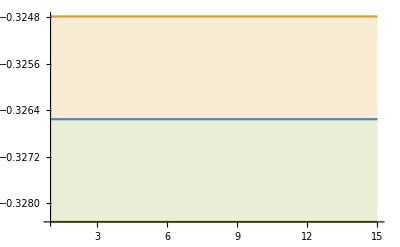

```mathematica
Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,15},Filling->{3->{1},2->{1}}]
```

```mathematica
SpoilHWFLOPlotN3=Show[Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,Length[meanErr2[[5]]]},Filling->{3->{1},2->{1}},PlotRange->{-.5,0}],ListPlot[{Table[{τSteps[[1,i]],meanErr2[[1,i]]},{i,1,Length[meanErr2[[1]]]}],Table[{τSteps[[2,i]],meanErr2[[2,i]]},{i,1,Length[meanErr2[[2]]]}],Table[{τSteps[[3,i]],meanErr2[[3,i]]},{i,1,Length[meanErr2[[3]]]}],Table[{τSteps[[4,i]],meanErr2[[4,i]]},{i,1,Length[meanErr2[[4]]]}],Table[{τSteps[[5,i]],meanErr2[[5,i]]},{i,1,Length[meanErr2[[5]]]}]},PlotRange->{-.1,-0.005},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]],markerlist[[4]],markerlist[[5]]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]},PlotStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau_{\\text{steps}}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3(\\text{mNLO})",Magnification->1.2]]
```

-Graphics-

#### QCD NNLO - gauss

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={393,393,393,393,393};
NWalkers=200;
Nf4α1LoopBig={0.4,0.4,0.4,0.4,0.4};
aList={1,2,3,4,5};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
csvData=Table[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"],{xx,1,Length[aList]}]
```

({mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.6898513610853985, -0.6882536326764502, -0.69532538696806, -0.6930790941095479, -0.6807079978100199, -0.6797191992074202, -0.683695017420826, -0.679387980010887, -0.6776417268386108, -0.7078901641797005, -0.7171637981186175, -0.7192502260711833, -0.7233648808248435, -0.7237967909955435, -0.7258515497524134, -0.7227642261305302, -0.7327305578754572, -0.742530959722006, -0.7341657457150147, -0.7682539759386642, -0.7492205050710191, -0.7464435200096012, -0.7494137416659078, -0.7908942624447238, -0.8113280859255556, -0.7959722051406667, -0.7856827469843013, -0.7512852598739033, -0.7862236784761043, -0.7660037111412715, -0.7956825397984472, -0.7740454510903503, -0.7664602155125307, -0.7470249195010069, -0.7601865838953682, -0.7405913066592256, -0.747722278203842, -0.7432964442372187, -0.748815054798653, -0.7450736953802751, -0.7517280436039178, -0.7252964686104189, -0.7369649255215239, -0.731918729486712, -0.7258824235618008, -0.7114192201678918, -0.7553524295840934, -0.7844824179748894, -0.7609371226169385, -0.7432492494520014, -0.7459999648715027, -0.7571857374160007, -0.7914787105004409, -0.7894042221871608, -0.7593412022804295, -0.7365454558573519, -0.7466707601610139, -0.7261459417655168, -0.7461678968045051, -0.7551824647672937, -0.7449748520241064, -0.7429065113570017, -0.7323127939396388, -0.7306725147288804, -0.7291547151089236, -0.7262394325813164, -0.7101730410248438, -0.734527168791071, -0.7251993669848162, -0.7464111029503078, -0.7494428827088436, -0.7477707748341024, -0.8348120438690577, -0.8617447287118182, -0.9095239179633211, -0.8469612990602273, -0.8882901128871292, -0.7760284202844029, -0.8017169602108968, -0.8162340766820799, -0.7686975105550093, -0.7837001125844631, -0.7245891669654514, -0.6940132168051922, -0.6706566666811509, -0.6676965387823811, -0.7217733671792443, -0.7252986499104022, -0.7282491723243215, -0.7339264312581992, -0.7621874330479602, -0.745189124583405, -0.7248411439127587, -0.7015728984284743, -0.7270091557535175, -0.747842128279047, -0.7268157471658369, -0.7516175167579954, -0.8046340487884541, -0.8228062989290287, -0.7894613008240734, -0.7661564749739719, -0.7665711949025279, -0.7691519524883517, -0.7829508367843022, -0.7665147806284314, -0.7155297596558996, -0.7338906297672798, -0.7250009549818707, -0.8107787462716659, -0.8628397262166501, -0.8097051127197616, -0.7611083924719332, -0.7875064615020576, -0.8014554829738887, -0.7748799927712073, -0.7753904546788621, -0.9052914449105298, -0.8843127277158365, -0.948316639936387, -0.8326726527665934, -0.8478728824958941, -0.8359970420720545, -0.8277160842510912, -0.8125425369567606, -0.786162290881967, -0.7901338892085977, -0.874799886677729, -0.8750919808400915, -0.9010091263072, -1.030580849938094, -0.8986512931873857, -0.9201566842362056, -0.8522674732747799, -0.8152259568835352, -0.8127645422528348, -0.7789521725060737, -0.7716821982160569, -0.7481542602841424, -0.7948200653946117, -0.8629662852610867, -0.8553019860242985, -0.8434914958102592, -0.8305640277829686, -0.776262802148629, -0.7588699796349552, -0.7518767075188021, -0.7573381912067187, -0.8229741446558201, -0.8154086454206896, -0.7980433341211914, -0.8076487927695488, -0.8142729089172204, -0.8208547483784415, -0.8258021067911259, -0.9128610725283888, -0.9886936661102106, -0.9923870000826946, -0.8910665414669201, -0.845116614189772, -0.8623702734529404, -0.8845686582677336, -0.8118027486317178, -0.8808417889921653, -0.8510079667836006, -0.8454537383089444, -0.7930251390223108, -0.8030754473460071, -0.8220900100444385, -0.8671967224487087, -0.9640914758493309, -0.8198119468284786, -0.8332931780603211, -0.8155635301494536, -0.7967139635161937, -0.817000209530534, -0.8373995573610772, -0.8932496082777353, -0.9194920603048831, -0.9974438415430255, -1.0116357829749563, -1.0018421173721836, -1.032637792252095, -0.9556099693266312, -0.9511330927011349, -0.9090393238359412, -0.8365973909412401, -0.8498120192039159, -0.7599191663059748, -0.714714370915072, -0.7178958638914877, -0.7534221521129624, -0.8402704953334387, -0.8004016485520417, -0.7664411305807886, -0.7470712320262725, -0.7295952280810646, -0.7089375301117581, -0.6762179288785669, -0.6763512791070251, -0.6852301353838255, -0.7044858087166853, -0.6829365843523283, -0.6561669875050136, -0.6495452410154697, -0.6385537272443167, -0.6591058790965139, -0.6414900626155873, -0.6426979685564086, -0.6694014853196223, -0.6680878793841926, -0.663385699862135, -0.6395871850152136, -0.6340054419711137, -0.6322259158393255, -0.6427236922339015, -0.5977485275711264, -0.6126176044253218, -0.6661550658671072, -0.6836089515731641, -0.741160440867667, -0.6597806957240038, -0.6772608762286744, -0.6711328153523639, -0.682611894635796, -0.7175543512456468, -0.663865262882408, -0.6543763319895562, -0.6914376826398675, -0.6686616796564038, -0.6825783521986096, -0.7057176550072518, -0.6975785687083684, -0.6719730453610017, -0.6850907896579418, -0.6450510589361136, -0.6225289431103764, -0.6186956060296563, -0.6268347927268038, -0.6181598161455705, -0.5964887197153236, -0.6225113827718416, -0.6120472922138956, -0.5937723347133779, -0.5909590855686512, -0.606799060744017, -0.6238719417942007, -0.6168854570311841, -0.6260973284919293, -0.6124002347191954, -0.6028094191438655, -0.6177032660320969, -0.6138525754971597, -0.647599883111955, -0.6221945266478713, -0.6015329851958167, -0.6110260645787151, -0.6173616960175533, -0.6001522601628814, -0.5958452593967737, -0.6213398133901831, -0.680199309388267, -0.7043781128011601, -0.7722944829397008, -0.7249340312755584, -0.7636024287708044, -1.1033757174948022, -0.7336020031963243, -0.7807194779573449, -0.7273482490994684, -0.6501498626589302, -0.6598312065968301, -0.7242776316120582, -0.7468978711894316, -0.7522958844534957, -0.7535120957833193, -0.7099075417754735, -0.6927499038951953, -0.7006552607909301, -0.6922186523163186, -0.716753016133341, -0.8057164004010741, -0.8623309427803272, -0.7900890191923275, -0.7775409910118368, -0.8346400407824014, -0.7717396095885385, -0.7830796438298463, -0.7615459060529685, -0.8080614342070629, -0.7783644097209874, -0.8197498796804432, -0.8698425321185407, -0.9458924309271626, -0.8975419383086903, -0.8969104439546249, -0.9528676126800463, -0.8329673187532719, -0.8879518089959848, -0.8224779996305785, -0.8026037982276519, -0.7814523202010373, -0.7200971830023196, -0.7146432576270345, -0.7677365486055899, -0.8834284236464931, -0.9219063977189317, -0.9887264120305631, -0.9536239591724902, -1.0909117828839225, -1.3092769951337455, -0.9519912135279865, -0.9307194969362055, -0.8281860741510962, -0.801732514240314, -0.7092742870813893, -0.8367458883070742, -0.8510860967379869, -0.8433674216270796, -1.0407378677028838, -1.0149784340298262, -1.0537834083562214, -1.055170628158419, -1.0248797358211603, -0.991719731774419, -0.9498869730606859, -1.043847807888768, -0.9683095993464265, -1.1930332603527416, -0.894025504545119, -0.7473983431166136, -0.7579603740483775, -0.7707270569634659, -0.8847488584531272, -1.0260271812255553, -0.8833247683286096, -0.8339907121272837, -0.7520273717420647, -0.7227419991449153, -0.7074244832047132, -0.6795173428504702, -0.6123257674664814, -0.6387446302114312, -0.5936177198359134, -0.571985637577172, -0.5992971066883352, -0.6373460090549069, -0.6584652865463588, -0.6566958215157674, -0.7491744257413807, -0.7707617893838935, -0.7308737540689332, -0.6284707141140987, -0.6251668371648954],[0.014106967706801303, 0.014094810695175299, 0.015695960653595954, 0.015228135434636548, 0.011038870382300729, 0.008677994417638151, 0.010244377510871228, 0.01075422087195094, 0.011245985690498943, 0.01789154290529099, 0.017308494736392274, 0.017524339821038154, 0.014812735319916222, 0.015116608244482882, 0.014850114506505665, 0.016120691170933094, 0.01959882934052614, 0.023873100474252312, 0.019557972550474673, 0.03632617034225488, 0.022660378302563212, 0.021537230093472175, 0.023036040888637775, 0.03225988743658984, 0.03836348612062053, 0.039467267841683376, 0.034619757535780164, 0.024524420085203384, 0.035643631153788484, 0.02752959220752302, 0.038209886055642475, 0.033596997080384654, 0.03083891979201216, 0.026498509948124856, 0.02884480839302653, 0.025301149618422315, 0.025054234358466817, 0.03461225912838835, 0.028321845977012847, 0.034089592444811405, 0.049223170111484284, 0.04285678268520627, 0.034419508823892477, 0.0289454264508156, 0.0392365280193618, 0.02449417978537364, 0.040373272069664484, 0.04568144145322533, 0.03369584158764408, 0.02022427477720246, 0.0204253030514953, 0.02414785009900919, 0.044832916036290374, 0.05822895725212183, 0.048223259211084106, 0.034639009841225074, 0.034326435976332045, 0.033908804734241724, 0.05084133742672774, 0.0601007956141689, 0.052897588678191824, 0.055331472371541825, 0.03913851564648848, 0.04751395141837918, 0.03918595217712062, 0.03923764537856222, 0.030772543220978856, 0.048396501554757006, 0.04658040230505234, 0.05491269174960102, 0.06425454513962905, 0.06815111196598991, 0.1222375253950485, 0.12361961954465805, 0.1431913272285808, 0.11805121415332843, 0.12970183716639513, 0.06498830952357613, 0.0805983990137242, 0.08773722399159928, 0.06427269086218201, 0.07516624209323264, 0.03424545116895158, 0.01678856558842049, 0.007704175086982964, 0.014932787763851327, 0.02001581363943543, 0.02573114099762713, 0.027972274396764578, 0.030849777580614, 0.040821536255934036, 0.02675470547378706, 0.02341684538109772, 0.02435724156826738, 0.02724117345083609, 0.03200646412130398, 0.01957798224781779, 0.02753013340357323, 0.05314929832508458, 0.05603316470786231, 0.03534799534770695, 0.025014157200812914, 0.03353814861872159, 0.03299638338368745, 0.0390446690228769, 0.03080154773300185, 0.01369539796636643, 0.017391218004558617, 0.014883901650378789, 0.05820829737200292, 0.12247084001347883, 0.04591503475187135, 0.03900599029552531, 0.03297133229883433, 0.04109477785336327, 0.03303125804358847, 0.03219360677327834, 0.07625798212111594, 0.05230057088655522, 0.07564761562200907, 0.03078062839789694, 0.05995597683415274, 0.04715664423747743, 0.04534557580584452, 0.024139310836566317, 0.029222266326672772, 0.05881306478832252, 0.07947561793684053, 0.062290680871513536, 0.07031928002129408, 0.0921134992472259, 0.05391509852422652, 0.10018347965957822, 0.04021621543383174, 0.054117544693913174, 0.06692963084517109, 0.09570071944624435, 0.10425709535982666, 0.09938691197930882, 0.069241620249744, 0.039007798025090294, 0.028909279293426418, 0.03710061620432192, 0.02156112387066518, 0.02073274515244264, 0.02994494895000597, 0.029927526089274823, 0.03913500821932055, 0.03928574316996887, 0.057874672703331353, 0.11000397969691524, 0.07854772486266078, 0.07010840529734247, 0.05300535312245355, 0.06445037879968676, 0.06782041830999797, 0.08388953787743145, 0.09870079596507103, 0.07652960801442621, 0.10157400652475732, 0.1877090685263373, 0.17939690929584232, 0.0929620441506453, 0.17662397241026834, 0.12955453422001711, 0.07588443764205714, 0.051144364632841256, 0.06402837634717433, 0.061390004447437654, 0.08093640448981797, 0.12745269060659223, 0.052632311555478886, 0.06304249187102245, 0.0622867555592072, 0.04845837399739273, 0.0704339906278493, 0.06684986160956526, 0.06568451514597261, 0.06718235978163495, 0.09217951157561516, 0.09744116651144948, 0.12231644630457969, 0.09675494116482868, 0.11153389391732985, 0.115831818894307, 0.10561723563217006, 0.07229592317646018, 0.08483380306131469, 0.025823262367160534, 0.020398501447216288, 0.012889994073102413, 0.024976940461717993, 0.07363198845973198, 0.043791549314531365, 0.03001775720938, 0.021630261927733135, 0.023141397464555163, 0.019162851921268067, 0.012870344029161063, 0.012132025864036293, 0.01454220932002206, 0.02317204759747426, 0.018821763609272422, 0.031513824141609297, 0.02057727988706938, 0.016287185525888905, 0.016178918325286326, 0.019443478911852857, 0.009294642007080751, 0.013628199038266932, 0.015408737955479838, 0.014200887837069492, 0.02259701948511022, 0.023508358209226126, 0.03801567836846244, 0.09845540251699918, 0.033769146619717236, 0.02646391887260965, 0.03206515512117273, 0.04169715798659251, 0.06789856300263053, 0.01999473401607537, 0.02013047300617807, 0.014665826064528573, 0.04462372423308136, 0.07377512088657108, 0.021790618363600273, 0.018254149500070222, 0.027695737956527324, 0.024356850625022974, 0.023868005406682418, 0.03384608777114889, 0.03180405223774721, 0.027834076766847852, 0.033790052301816156, 0.040336557961090244, 0.04027621197174031, 0.03738742378550484, 0.05371097188441933, 0.0427822511321517, 0.029233186420077144, 0.021150457629823295, 0.019896901954781138, 0.026180273827200708, 0.022096278160959947, 0.016875251688440916, 0.025162530346186027, 0.028465761019756192, 0.041958219021778355, 0.03408372016986128, 0.03758844413549536, 0.036235724695801406, 0.03218426748362986, 0.03643427024389182, 0.034685788781629055, 0.0364992865104855, 0.028818559075932303, 0.02984714895727832, 0.033523574262433575, 0.03488209902037314, 0.03634109539592434, 0.07845450503406787, 0.09836188415325986, 0.1462647497031246, 0.10831142942846653, 0.1268369582217241, 0.35360105972419725, 0.0986999906652341, 0.11977862221780669, 0.07961417745612341, 0.05011469441112974, 0.05834383602541362, 0.08908180975015909, 0.09228668135624056, 0.09396887665646177, 0.09397381528868883, 0.06929560213902242, 0.05886941534511057, 0.06272130739111302, 0.06803608059896434, 0.06613870849692277, 0.10546856735452743, 0.13002322246327946, 0.09529328643333992, 0.08700434425476283, 0.109343457488931, 0.08007322866554721, 0.08452532160779402, 0.07657110687821124, 0.09364642364467976, 0.07758854107373554, 0.07541296038527151, 0.10539076789929236, 0.1321074505207256, 0.1287381091054601, 0.11031830282124183, 0.14364460032306478, 0.08392436888363047, 0.09643952774277535, 0.06455498501223506, 0.04985426720429692, 0.04448112987018346, 0.02211005567158915, 0.018784198721008196, 0.05024036002934541, 0.09654241198687595, 0.1093812694713194, 0.1525879513895896, 0.13200477392601237, 0.20944315409839903, 0.3020574866125412, 0.12318123213201813, 0.11377878487679285, 0.05550501878658974, 0.04178134639171654, 0.01824604945513949, 0.06420047356381581, 0.07127243360888974, 0.07362553118287218, 0.1522620618717887, 0.15104284084568162, 0.181379465588251, 0.17712965924456997, 0.16174414057284017, 0.14092194078071021, 0.12846840395695164, 0.15974870636438515, 0.13006915822328893, 0.24055333125003636, 0.10446458890991556, 0.046647785838103625, 0.03825597419010742, 0.04212953520727946, 0.08541453770096913, 0.1682902536539441, 0.10844165683486758, 0.084552242418677, 0.060434343302589816, 0.05466546104005767, 0.04563366146798095, 0.04686505542762416, 0.03861842108342523, 0.02568576499740501, 0.0455589130717382, 0.04978222011461163, 0.035162802571237294, 0.021436245009164166, 0.03152691361983314, 0.02304707757850737, 0.059233664508428985, 0.07470132391394599, 0.05217675840782767, 0.017477076306479628, 0.023299333027220266],-0.688164,0.00194315,1.35978}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.5299726625521989, -0.5127826070788623, -0.5206149234388502, -0.5101221014801776, -0.503881499091413, -0.5069624846727316, -0.5199067633149083, -0.5174169245509512, -0.5237820349050688, -0.5208212679402678, -0.53898048794817, -0.5392950664684804, -0.5588234066270622, -0.5623145739122842, -0.5806924830735459, -0.6041016001912337, -0.6319274323790253, -0.6486164247874253, -0.6284344485913729, -0.654394209892662, -0.6583099838489198, -0.6241925662619665, -0.6353210689811786, -0.6231731998557168, -0.6445687967937223, -0.6567642552941116, -0.6656704079918091, -0.6655530021000953, -0.6748399201317448, -0.6671484195576372, -0.6610058000486739, -0.6493661765086679, -0.6562463464983198, -0.6458105730101505, -0.6640820447492638, -0.6411166582451279, -0.6508415619572829, -0.6328503968419965, -0.6245550887437427, -0.6255222749671732, -0.6248455764738323, -0.6216091983413109, -0.6313768733060485, -0.6000168011696361, -0.5879950362300749, -0.6052512344309967, -0.6107875174950183, -0.6082807566940854, -0.5966025373286749, -0.6066378659093975, -0.5913414514622402, -0.6018676936551435, -0.5598481690806988, -0.5580697100117301, -0.564662761538725, -0.5583812996470384, -0.5588646066083374, -0.5591652393587325, -0.5505797672817235, -0.5383520342421492, -0.5411657590191821, -0.5499941416418449, -0.5483239185873429, -0.5521111999257161, -0.553585569081739, -0.5517805167045089, -0.5495592172641455, -0.5434564363940656, -0.5456735977113093, -0.5482029315694344, -0.5358074974911226, -0.5317779427277982, -0.5344674375911092, -0.537323044918501, -0.5430590061374513, -0.5581451208459131, -0.5724313316354526, -0.5682972085706222, -0.5497277196698727, -0.5520945475996691, -0.5488941915975727, -0.5477957961136974, -0.5380287102658421, -0.5367550012757886, -0.5311312253531415, -0.5276939308892646, -0.5312142320570081, -0.5458147763608141, -0.5442329261539731, -0.5305979589767558, -0.5442517316262152, -0.5391483432409647, -0.5281808162975717, -0.5309378738873776, -0.5473933080569618, -0.5562296742812353, -0.5537340286033393, -0.5561183608444074, -0.5324511176334447, -0.5440134754843017, -0.5212979381733079, -0.5149781008459969, -0.5141454124323231, -0.5180385621694791, -0.5298983754302599, -0.5362539613238192, -0.528723857465965, -0.5332778961251143, -0.5385485131797273, -0.5417138895165775, -0.5356415706651484, -0.5181293020085471, -0.5271054627845844, -0.5218086710543042, -0.5247537900546307, -0.5202058162250395, -0.5172750288511879, -0.5220866360416118, -0.5292695038809514, -0.5383191194226634, -0.5317712805463313, -0.5247046865583019, -0.5332526417962582, -0.5301500599762731, -0.5175243023091288, -0.5210234823391261, -0.4991702230688051, -0.5287744570005124, -0.5137087008512436, -0.5074127265716012, -0.5137125257309723, -0.5138733704943551, -0.50275896194815, -0.4770899784673959, -0.47767398817124995, -0.47378089210901786, -0.4735583976608865, -0.4802132982413133, -0.47319991729053645, -0.46317935070274313, -0.46625548682235296, -0.48195121633378835, -0.4889849482204915, -0.4750941773135243, -0.46181350751149086, -0.45253361987643376, -0.4630252929922766, -0.4561995274188184, -0.45864716389366494, -0.45413084701486506, -0.4625499085518723, -0.4508681462143856, -0.4632898616555557, -0.46291792298718487, -0.47010553989411186, -0.4689025295478041, -0.45769822297661117, -0.4484448298859421, -0.4422424983871408, -0.4494981777694066, -0.45516385462969716, -0.46289993103443366, -0.47944802936557246, -0.48245015007994746, -0.49586559419390724, -0.5158854483585802, -0.5459188960561433, -0.5930360455559015, -0.5372187811514036, -0.539893534677539, -0.5465843667384666, -0.5368572239056072, -0.5299052540088537, -0.5474753964279983, -0.5699209573674558, -0.5584172732786568, -0.5703166232516491, -0.5778751805873817, -0.6183420255307057, -0.6063619429818693, -0.5626317621504908, -0.5568881306614847, -0.5953780092790228, -0.6409266561394961, -0.610975357952395, -0.5541108525076198, -0.5125861153741791, -0.5256102439520876, -0.5382818076875667, -0.5251029188565433, -0.4992939252561768, -0.47814154463286174, -0.47053277738817517, -0.46399112765241096],[0.016942637006046382, 0.018390243149224536, 0.020880574777764598, 0.019663061983772517, 0.02323727502489953, 0.02371900583419054, 0.0215504832543057, 0.024935160035584155, 0.02620330574209542, 0.025448281881565258, 0.018226618452722096, 0.017525099149898516, 0.014968019130852037, 0.01585745330946274, 0.023253926752789415, 0.020516502872868, 0.01971988983917563, 0.02637805421364816, 0.02562391694720855, 0.03883406455079164, 0.04304606352068036, 0.03221395702619927, 0.03705083823872642, 0.02124203964839118, 0.027482367152769548, 0.03022530301560883, 0.026871562737428054, 0.031319015095954826, 0.03133736241361681, 0.02500838506204131, 0.026094261062765894, 0.02553513696208598, 0.024369584621016478, 0.02614624712048676, 0.03504016033353306, 0.026178073675588092, 0.040674714582090626, 0.024202656040620572, 0.02239326315032784, 0.022992096650908025, 0.026301340322061526, 0.027393086220470726, 0.026997025920993702, 0.026392166118148586, 0.01637004367563539, 0.01789382908943884, 0.026950358888451802, 0.030081627588680424, 0.02983269501504312, 0.025857849003955564, 0.02286084864701768, 0.019787189736744266, 0.012160544130441011, 0.00849331346443388, 0.011552978615703927, 0.011797987419460886, 0.01707118640546445, 0.014826796320275348, 0.02230408491518317, 0.020887003923846376, 0.023738624882839832, 0.023952181074431086, 0.02009917666601828, 0.017403938603975454, 0.01908966256929995, 0.015227284813320942, 0.018490329548588855, 0.029923585729396036, 0.026912096490806014, 0.029589466698958743, 0.03919494574849331, 0.03230776040276716, 0.034649424419387176, 0.036116627636897346, 0.0369596081053794, 0.04644924631978409, 0.0699158995782075, 0.05997297960841777, 0.05070182077632455, 0.06445989446468747, 0.058039560285655684, 0.05234774951007231, 0.04387293547834672, 0.043452381723862364, 0.02795870174040796, 0.01911013600636014, 0.014524552529519492, 0.019857154866512256, 0.01929485009368356, 0.018439081866551965, 0.025472754685220998, 0.024871704069862777, 0.028405884566496478, 0.03257177973817961, 0.030082447687716476, 0.03051755578958438, 0.033202133007496006, 0.04952190143190945, 0.026437469006144104, 0.030276746370794694, 0.027418753812908182, 0.022668384622179856, 0.0220877292215128, 0.02683700995937795, 0.0340360121722044, 0.034147439288002214, 0.02897233918225262, 0.038720733474547034, 0.04521039354351957, 0.047136103839092815, 0.04423293544550981, 0.0377112612442667, 0.036521845230533076, 0.031746063737466315, 0.02868029335010663, 0.02653744178595933, 0.022374143987717678, 0.015675257802086732, 0.013792537013912282, 0.01392423921458211, 0.0238506162190583, 0.021803379383437342, 0.02787984100240242, 0.030918122157809536, 0.026711557093786236, 0.038712456600061895, 0.029892833340415245, 0.05148749800728903, 0.037776310868685374, 0.030721091963683212, 0.03370637307447463, 0.03601697972250869, 0.02947039194359297, 0.02030444204576117, 0.02420499308175174, 0.024985958005439027, 0.024366742892694176, 0.021668730774105333, 0.015637875208217907, 0.009652782596377623, 0.01209703540989923, 0.022773104025860864, 0.03338455182078546, 0.027859746660771983, 0.0254873473437933, 0.01723964688904865, 0.0233832290687975, 0.023874674829758823, 0.022202060379844138, 0.022435835937393418, 0.025574059844839663, 0.0200543150427102, 0.026170251420212697, 0.025715469189013938, 0.030394251442071116, 0.02742618694091467, 0.021577114211321632, 0.019102907287928687, 0.016425146371879473, 0.021261507328850366, 0.0255279086201301, 0.02979448267812737, 0.04057200863795414, 0.04103605337830129, 0.050038715004844685, 0.061421633665031845, 0.07620667392029068, 0.10416481227186372, 0.0658789786515299, 0.06598050864740111, 0.06950490443365417, 0.06860287406331499, 0.06564486695880999, 0.07439935589571067, 0.0833271557372025, 0.07483387872182848, 0.08062069261917255, 0.08537664999164607, 0.10293689918628071, 0.09821843150564724, 0.07634385818030964, 0.07073446988224316, 0.08661532126797064, 0.11301162008601859, 0.09711611389117022, 0.06435938975580852, 0.042974351196141285, 0.04469657289111511, 0.05162589140699269, 0.04310791109445991, 0.02915260734583488, 0.01517455421858407, 0.00953609333450371, 0.008828203271194402],-0.523224,0.00232534,3.48239}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.4284006073574499, -0.42804575406521206, -0.43438491680067315, -0.43934207875516074, -0.43920230952462547, -0.440147562569433, -0.44085980938813396, -0.44628871942078147, -0.45360271215767406, -0.45747458711853595, -0.4660782313778915, -0.4771452797155751, -0.48417517217949624, -0.4865423596871721, -0.48925301237356994, -0.48976735166172713, -0.4836725621797195, -0.48353682341977466, -0.48702976845333107, -0.4932673813454008, -0.49776847040075095, -0.4977202908968601, -0.5035985187290027, -0.5079304508081403, -0.5222172935931116, -0.5085917512952093, -0.5031806484857095, -0.49935362110471637, -0.5034285953799474, -0.5130808300461318, -0.5104127059515823, -0.5166129007089555, -0.5274095508031745, -0.539380415632658, -0.5576539926150424, -0.5552937282066842, -0.5543804698867777, -0.5623097748930966, -0.5641513543665555, -0.5793971164725402, -0.579802373286504, -0.5813075990155618, -0.5863635819433166, -0.5921608722932362, -0.604220877036933, -0.6189406419309685, -0.6109390238978873, -0.6378487903333775, -0.6408473837777846, -0.6185726734407243, -0.6291182230197948, -0.6266624234705186, -0.6181213510293317, -0.6140848617991067, -0.6089562337828476, -0.6133189063156422, -0.6043131075700082, -0.5951291695697363, -0.6002823884275535, -0.6346557211162737, -0.6329054821925422, -0.6547323062083573, -0.6751309326504732, -0.6638236244373309, -0.6526631049930769, -0.6564346215392847, -0.6324864818883691, -0.6421137685652522, -0.6623486867689481, -0.6985808312491014, -0.6760441274299903, -0.647124790407468, -0.6577043683664361, -0.65249006445111, -0.6409605374326708, -0.627452841328488, -0.6451702531678107, -0.6155690038137345, -0.6065414710497711, -0.6060150894435863, -0.5965038565245266, -0.5994814311953477, -0.5904518265888895, -0.6152124849449435, -0.6462419247566226, -0.6509012292790765, -0.6286931029443307, -0.6391689511496319, -0.6446748387324643, -0.6687215974670689, -0.6525497471965307, -0.6488628203718344, -0.6474651909450667, -0.6594392699277456, -0.6621326668545626, -0.6445080120306531, -0.6311701292253794, -0.6382051124992866, -0.6380499573574683, -0.6327325058456343, -0.6472612503120296, -0.666465764514903, -0.6625092336103974, -0.6426357548457057, -0.624383547689096, -0.6098526972054108, -0.6138058776058625, -0.627199521018265, -0.5955734430179849, -0.5768996947777394, -0.6001087286187813, -0.588082516431368, -0.5896829881356839, -0.5918640888579699, -0.573886240747432, -0.5505494066333338, -0.5473505715273116, -0.5465232725465625, -0.5246450606214519, -0.5347133092624811, -0.5366770274142836, -0.5472317569672284, -0.5311479430573239, -0.5282031735451308, -0.5424842780793425, -0.5631126471951964, -0.5616051535542677, -0.5733463343028482, -0.5901202585733144, -0.5839830751259258, -0.5600782882939874, -0.5565530652015304, -0.53881710183176, -0.5228721296898371, -0.5064197395764074, -0.5119018096543761, -0.509774646548302, -0.5164837930221555, -0.518072856938593, -0.5098222668022674, -0.5253482324646738, -0.5384667575934324, -0.5391191181366018, -0.5408733697159259, -0.5502709102168092, -0.5574934962523221, -0.5593094782067338, -0.567547236672458, -0.5594618814471563, -0.5664044144180304, -0.5862177645382808, -0.6019733793654367, -0.577662204293039, -0.5925294004383255, -0.5814416107040211, -0.5735862146355876, -0.563900155837887, -0.5816228593351741, -0.5755579166047883, -0.5503940325517044, -0.5261949790737983, -0.522094252243468, -0.5075477186324306, -0.49099589475275607, -0.4797723200775013, -0.48940073009870233, -0.49114456127536527, -0.5149592566527565, -0.5278286207465854, -0.5307285317404293, -0.5189145010001283, -0.5160581037160011, -0.5219425580614, -0.5082297037569492, -0.5126203265389521, -0.507479057478388, -0.524473099469993, -0.5251993186670038, -0.5357838011875652, -0.5324252861394355, -0.5293894482410053, -0.5285875676979758, -0.5482136178544842, -0.5632601894712534, -0.5512224093284838, -0.5539426620801134, -0.5434394208968408, -0.5520720316729935, -0.536232186323813, -0.5166909783423916, -0.5201025259804034, -0.5254511410838212, -0.5195838791914135, -0.5256152825539965, -0.549023982770126, -0.525243904489046, -0.5248149967111322, -0.5154889817850256, -0.5127306931933637, -0.5062554941532453, -0.4989589298836952, -0.5100103265658262, -0.5183954324379114, -0.5002582629676647, -0.5022745744862342, -0.5197753059658401, -0.5150894041646535, -0.5043218997673925, -0.5035639812058146, -0.524100001164972, -0.5096725192975641, -0.5136487010789687, -0.5012453093130271, -0.5117027592344141, -0.5196726222804016, -0.49078735706468246, -0.4772280774369907, -0.4628469971985342, -0.45136814986853563, -0.4492748012272953, -0.4478234894520753, -0.4508727862415183, -0.44993625891165384, -0.4573257723665117, -0.46027886271687335, -0.4617880865136621, -0.45534051390735664, -0.4577426285449598, -0.4538175543121786, -0.450655007986813, -0.4452678070932285, -0.43934184514310115, -0.4492048918940792, -0.45565856206788363, -0.46356411826715815, -0.46662167328777177, -0.4716783806531313, -0.46417798669388555, -0.461842316148358, -0.4549881908962937, -0.4672885665401807, -0.46253221780871057, -0.4589552027407304, -0.4607040508503654, -0.45615572582798936, -0.46028185564056895, -0.4616840011333844, -0.4570405839045632, -0.4562338007754957, -0.44517265191560723, -0.43899832734389355, -0.4393036183516935, -0.4283475138047256, -0.42666829502085796, -0.45057638116729587, -0.43476471929786237, -0.427385926759377, -0.43021222489239186, -0.4308725638967533, -0.4283878725336336, -0.41320772384524446, -0.40413350312928453, -0.4052337306809715, -0.4035360754249051, -0.3989686566591619, -0.4012460342784258, -0.4058099323533341, -0.40064584601738573, -0.400911795127652, -0.40294288618287954, -0.4039022229296812, -0.4006871481023391, -0.4075138943961485, -0.4090363113200021, -0.4072589213950323, -0.4082707496263854, -0.41377482938876153, -0.4244054864339858, -0.42990491334320974, -0.4334133653017679, -0.423039079635427, -0.42877614686173715, -0.43464565173815073, -0.4275417279319498, -0.43033213536096154, -0.42715678948954544, -0.4270339288030393, -0.41746960499941366, -0.41634012660959596, -0.41709767177489304, -0.41893610805553044, -0.4215265976231399, -0.4215857941063155, -0.4172343626503724, -0.4119878845249989, -0.416144322087016, -0.41369764401678283, -0.4147409096347415, -0.42353872786968094, -0.4176834543217835, -0.42412904909621735, -0.4245950066149005, -0.41847543628168515, -0.4214882704536921, -0.4218506398910267, -0.4192403309968008, -0.42272183790970796, -0.4245037823804098, -0.44366641353148506, -0.4422183053670814, -0.43679525190456037, -0.4428389967787433, -0.44926290620486625, -0.4454735239662161, -0.45904846565834434, -0.4650915515677371, -0.4724807518189366, -0.4763998773256851, -0.4659796661492919, -0.4574282231883116, -0.45517708169209586, -0.45519708439382023, -0.48490046443846063, -0.4964079562455303, -0.5041551709047156, -0.49740640820209786, -0.5279791519693179, -0.49065791958756905, -0.46678983154279935, -0.45326268580816703, -0.4507568081225207, -0.4384589798761628, -0.43025541658726596, -0.4279519584926846, -0.43285170349366225, -0.4372418499605411, -0.44644530149514866, -0.44111492764995386, -0.4377909941409479, -0.44264315398106235, -0.4432261572549114, -0.44304658257311996, -0.4428886733785805, -0.445771130592765, -0.4517380766768414, -0.4522642704079797, -0.4500324271124603, -0.46080140080062265, -0.4628063293842002, -0.45763048986139876, -0.4580397100887142, -0.4625239517694018, -0.46901912783827104, -0.4551191987645207],[0.013691783284775593, 0.013451617963759523, 0.01499085085964393, 0.015903219549101417, 0.015966499636254, 0.016458132982855117, 0.017334973716204564, 0.018241165125206456, 0.020130964281444227, 0.022337910587134063, 0.02649712262632929, 0.03111622363880358, 0.03433013196221789, 0.03454489982203561, 0.035365372798922885, 0.03187743636194073, 0.028028548121711645, 0.027227428124644543, 0.026689856816281984, 0.02640899016848523, 0.025646734013970985, 0.02634538548432512, 0.02879521959266645, 0.026185972707410115, 0.031026672550301563, 0.025657992816229384, 0.025915250820533232, 0.025721889593675298, 0.027345108551655114, 0.029145063167149717, 0.029489592225920576, 0.03172043650069312, 0.035222953483788726, 0.04192974121856356, 0.04918665882207835, 0.046517768119370535, 0.042978092669735214, 0.04188530042205301, 0.04239205759027905, 0.045167536105732355, 0.041633111712395955, 0.039347658931985004, 0.04015956276649237, 0.0407357978099789, 0.04281897799851421, 0.045660156641165475, 0.040301484898209256, 0.04653114883744937, 0.04674899889753964, 0.03814066640272884, 0.04215192235029243, 0.03872599418096406, 0.034158421116416884, 0.0327957606685041, 0.03249991789167137, 0.031469304366944784, 0.03287105120410808, 0.028947986847961564, 0.03044447882715465, 0.04490633909720327, 0.04093490072214569, 0.0380485630941319, 0.04236204287801293, 0.03950897585985879, 0.03740224738586724, 0.04115872615733094, 0.030199704760979572, 0.023572668892161315, 0.03066356215858018, 0.049900997138049664, 0.03372686578140834, 0.024655362393142782, 0.03417702156447163, 0.030173505650483413, 0.02960843964187949, 0.028176366379352318, 0.03434377906377894, 0.036728103279649524, 0.041669380025427, 0.04103306961081814, 0.03962265955912499, 0.038383488830385205, 0.03685740426728317, 0.03942493408591517, 0.04753060010420003, 0.053444715446546616, 0.042828788284576924, 0.04268023504393551, 0.043789788034049516, 0.04756613321438875, 0.039116687287001316, 0.039425482802224576, 0.03927802804729165, 0.0436456184754429, 0.041943448794879656, 0.04567408385900679, 0.03279159347341741, 0.03391087867130824, 0.035911634646933324, 0.04088717182731746, 0.039444575465915774, 0.04848132567839233, 0.04336935187823673, 0.035449114810534796, 0.02923428974253238, 0.024951991336871655, 0.030688987740535235, 0.03961274375780484, 0.024406856755657465, 0.029982000267670773, 0.029727259333723832, 0.03029699375808409, 0.03078625725476561, 0.026592321444372787, 0.0244745053006821, 0.01670164289085006, 0.016512824107911432, 0.011239794444697618, 0.01293123857951149, 0.012131624100671576, 0.01478809510949318, 0.01316973060483196, 0.013294413037269538, 0.015407929979164637, 0.015929235490100436, 0.02118636515440348, 0.019671425474911873, 0.030380777116433406, 0.028802211609565472, 0.031021082373375915, 0.02660215545300188, 0.033013407799716364, 0.029755223261568067, 0.02900840490128274, 0.026966965433626276, 0.03543769723538417, 0.03167599125321367, 0.036880858734931986, 0.04113203633385837, 0.047032546891561826, 0.056419053228100126, 0.0657708711554093, 0.061249633271211114, 0.06416238644720526, 0.07962266665599574, 0.0737919643405585, 0.07394827275483609, 0.07648591072101295, 0.07412390140871455, 0.0761213168656623, 0.09003435232892266, 0.10552162221928656, 0.08835173981691806, 0.091722945441701, 0.08636945442051133, 0.0837865241471745, 0.073073673626299, 0.08361357381332177, 0.07256458175881157, 0.05533303298023449, 0.0403017700954959, 0.041040891974252404, 0.0236295841791531, 0.01854886051041346, 0.016640276247942187, 0.025137651854364305, 0.023084013072693678, 0.04300598340978825, 0.045090052287312055, 0.04924957277289714, 0.04863592342449776, 0.04403384132843468, 0.045725460645590014, 0.035018732587770995, 0.03519529428899798, 0.028452442355645015, 0.033962511506149165, 0.03432381148884576, 0.04193127098188425, 0.03953802498271973, 0.04217766206024417, 0.042939908098391016, 0.05302820073671785, 0.060399834054166344, 0.05283236035618451, 0.051838612588471306, 0.04318150799953288, 0.04531860599954955, 0.038947628294995575, 0.0253240082571982, 0.02710592156118622, 0.02893121336962806, 0.024856600337369254, 0.03793764681712666, 0.04996221233757403, 0.03671899983190313, 0.03786911503668419, 0.03283066070796935, 0.03142081249598925, 0.029293896053896786, 0.026310478061716, 0.034837305507190615, 0.04076258988431459, 0.03357908559864429, 0.03546362275872594, 0.040075019199308254, 0.03481943647546078, 0.03173561464106278, 0.033196546806294, 0.03628261157456497, 0.02859001130532938, 0.03153832267441671, 0.027194932920854172, 0.03476384055999083, 0.0372674136407293, 0.02434351521642894, 0.017022556514292176, 0.01057876039343683, 0.011231297849946963, 0.01234132075500251, 0.012707526357042621, 0.012118046904444065, 0.013409783262201843, 0.01314709049171657, 0.014582956146614603, 0.015069885278175781, 0.014099734731664471, 0.016691031017879193, 0.01988293615613939, 0.027810498877016875, 0.027290681854385983, 0.02940629273095889, 0.022133497116698018, 0.022280658741670754, 0.021761059063371755, 0.021998622581467318, 0.02490724380011122, 0.026115637957110163, 0.028697076647301978, 0.0351460631561695, 0.037176105773563645, 0.0480425112476617, 0.052185393607496786, 0.06288140214717938, 0.05039083188458681, 0.036708110354281474, 0.04053869029234632, 0.04731055274833443, 0.03152761807712009, 0.0340918947778979, 0.037771811819805545, 0.055345132497675635, 0.05640273719934967, 0.07315159208203284, 0.14249588850393713, 0.06675310491501174, 0.05527255801153321, 0.05348994010657627, 0.06148777965833646, 0.05219737153030265, 0.049568293125823344, 0.04274473536390554, 0.041043369898235676, 0.04007602265299584, 0.0396744997762343, 0.03818412971304877, 0.041064563771309306, 0.04624427894392045, 0.04568243370466843, 0.04308244311455236, 0.04562893935428436, 0.05059877050090734, 0.052781159787691004, 0.058520780353472746, 0.05476706693059434, 0.04953659528439492, 0.05129702141212305, 0.05171829017011732, 0.05287485754359884, 0.05138870490238227, 0.05381171625742855, 0.053145872753488255, 0.0608160237965846, 0.05162177347938466, 0.054391640076554115, 0.065538992423122, 0.07064355909399969, 0.06301078270626802, 0.05665005880066216, 0.05234074202834015, 0.052860839881135505, 0.053177141091997136, 0.04928016755002157, 0.04967108979692431, 0.04812189627997094, 0.047303327415142926, 0.044171697543696535, 0.041630374173895326, 0.044020737166877086, 0.03661680807122994, 0.039281158552122705, 0.03637342826697945, 0.036535747555174906, 0.038401755370035144, 0.040015957703867955, 0.038538196247972875, 0.04192932007773259, 0.0461968635169615, 0.05561968963717634, 0.05326846381084563, 0.047681953865248906, 0.04848137149047477, 0.05549591604620107, 0.05049070362201453, 0.05867970204375224, 0.058071615349467934, 0.05910927159005862, 0.05766882156786474, 0.05292123362975908, 0.046104902897741155, 0.04376728225093813, 0.04294469411319469, 0.06145168981667282, 0.07265756252817039, 0.07883279271938225, 0.07196372786478779, 0.08279971026886628, 0.05588175326496469, 0.041807241871840484, 0.03336233850809171, 0.03148384107892083, 0.028598301795619806, 0.027708062762177608, 0.02646771620496151, 0.026540921949519264, 0.028738523089730367, 0.030341972454518522, 0.029380175803862332, 0.028297695611868384, 0.029214136334361762, 0.030012612306107377, 0.028944898329865874, 0.03048420357796064, 0.029782986423118437, 0.028987772553065453, 0.028780527194822814, 0.030290097441438048, 0.03115526761806064, 0.030148750114784607, 0.029928668544204774, 0.030114054470381135, 0.02869799974328592, 0.030519505692087504, 0.025913239854325452],-0.499443,0.00222301,1.34409}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.3851200230065289, -0.38521393588084024, -0.3883517344518932, -0.3952676660738524, -0.40148404381476377, -0.409183375584356, -0.41352579608936213, -0.4338023186544923, -0.43300576668220325, -0.4228546379569458, -0.428882818002194, -0.4306876476844845, -0.4381940147719775, -0.44515918335201715, -0.44483362275220767, -0.44596493178678726, -0.4488856959386572, -0.44262270310837776, -0.44885901682932433, -0.452702457068522, -0.45233777271988584, -0.44995337294066234, -0.4484856941601999, -0.4511342575601113, -0.4565788485926161, -0.4663609839621756, -0.465828231558783, -0.46381599730108247, -0.4628902551497032, -0.46318433746144616, -0.46551683324178117, -0.46876117945323476, -0.47594483918546987, -0.47746655598393684, -0.4776779859134167, -0.47899477947047947, -0.4888991602002906, -0.4962174540329333, -0.49116231071659167, -0.4844677585266367, -0.4916343209796956, -0.49248139324005835, -0.486025214752707, -0.4856688809562638, -0.48496740605852684, -0.4935159902228712, -0.5103015832761697, -0.5075557329002476, -0.506207065115605, -0.5093604891707546, -0.5082426903548181, -0.504109516275496, -0.5014540118158448, -0.49818743266669, -0.50089867977784, -0.4851516817266947, -0.5008922459109897, -0.48870901688095897, -0.4959262083762338, -0.5093411651842514, -0.5016372697501172, -0.511235185091014, -0.5149995119242984, -0.5035995938844761, -0.49272058502239807, -0.4926616229784359, -0.49298885806455567, -0.4923304070694966, -0.4928611097655286, -0.4875096108692692, -0.4918136186377952, -0.5058507544936779, -0.5061719966885326, -0.5168009722634148, -0.5226051201056076, -0.5266063765439271, -0.5366158378514955, -0.5292258076528505, -0.5222681328899843, -0.5175034252257618, -0.5123091539729505, -0.5192329742772626, -0.528169393234709, -0.5358784845568393, -0.5387910163270088, -0.5215057584640114, -0.5294212380435612, -0.5297393347809062, -0.5381341921521484, -0.5500852508112444, -0.5333345753294412, -0.5443519465705277, -0.5294819850917383, -0.5261571138578556, -0.5465300419460687, -0.562315656822368, -0.5542001147780837, -0.5684869410817246, -0.5683549100143825, -0.5488709225247516, -0.5531468244828862, -0.5385071886139398, -0.5245569966258024, -0.5223926041481727, -0.5056147864240834, -0.49256143390636686, -0.4871778085101831, -0.4798882603611446, -0.4838204259925307, -0.4766421342577159, -0.4860173975999965, -0.4847553333866151, -0.48155988040093317, -0.482772145940142, -0.4748302914487242, -0.4718420938251351, -0.4772788799747585, -0.477328084060156, -0.48011345704121045, -0.48919515340824543, -0.47993746393848136, -0.48093461687394473, -0.48865982519623696, -0.4928835652499289, -0.4991771247484662, -0.4978866602903674, -0.5202979831354063, -0.5360068108544771, -0.5369422943987666, -0.5322285602755717, -0.521907316452692, -0.5316958180085807, -0.5185764739501108, -0.5219333063198682, -0.525397409813351, -0.5467760791228502, -0.5284170554979496, -0.522425860486111, -0.5201941220491602, -0.5458266157313731, -0.5501571376213001, -0.553836797394702, -0.5814189710018499, -0.5913631957784095, -0.5682911942110997, -0.584884990537607, -0.6063816756662509, -0.5899052829747492, -0.6199507455926212, -0.626533458441078, -0.6400723666254358, -0.6222370275514779, -0.6622014382922505, -0.7066951201340423, -0.7271337591640309, -0.662800975114552, -0.6667952801138591, -0.6466506248462851, -0.6586891504078184, -0.6942290127101989, -0.6711682602078373, -0.6207145586772884, -0.6464825893140422, -0.6134808455558727, -0.6002626338267671, -0.6499841091925839, -0.757668761247519, -0.7110925571530545, -1.2330146558579496, -0.7894455757551215, -0.72084539684249, -0.7426128840416898, -0.7104194077610143, -0.6980311014065607, -0.6664091704109502, -0.7014985629846877, -0.8404381966813944, -0.8619476402270517, -0.9199333193262045, -0.7183757056029766, -0.6790561022617734, -0.7243188491872259, -0.7272960884439695, -0.7313413787272995, -0.6816271872993895, -0.6745973824326267, -0.6412263779535279, -0.6359883351105373, -0.5980703325592943, -0.5660022018214242, -0.5588119051724365, -0.5620979699571171, -0.5648844461924813, -0.5586737256422444, -0.589311983968002, -0.5509757015099674, -0.5610641142387061, -0.5527602722176943, -0.5390537869158295, -0.5407076367984355, -0.5190269430452413, -0.5352630728514415, -0.5458979884313173, -0.5219340585256996, -0.5198634195514725, -0.5343767589745344, -0.5226835538873945, -0.5211720333300497, -0.5240861390324199, -0.5494226478767865, -0.5548145131190795, -0.5720463760055771, -0.5460155685962094, -0.5606024002963885, -0.5818836406731616, -0.5441683496810389, -0.5348011737994522, -0.5248693263219117, -0.5022142129912629, -0.5067361941946636, -0.506108065241182, -0.5153007251574292, -0.509975456225773, -0.5130081560813345, -0.5156043557752839, -0.5152050462643122, -0.5030373810664254, -0.5089180816772859, -0.5045068492038853, -0.49256821936397716, -0.48841724511636136, -0.47866647789684913, -0.49256805586197056, -0.49968218795932146, -0.5098677113527166, -0.516003857912615, -0.5246712717931417, -0.5106034739936646, -0.5044646089783181, -0.49643674357617573, -0.507342350187189, -0.49760746162967795, -0.49206848810865195, -0.4814136519775498, -0.48862371836041035, -0.5006699736776329, -0.5005319589650129, -0.49931600216346533, -0.5148838858319444, -0.4943923724983363, -0.4809963172214972, -0.4754171922222122, -0.4525663559148607, -0.4463516673761271, -0.4577879732331914, -0.45786619261794564, -0.45278246215983436, -0.44899952079132693, -0.44861251227542204, -0.4469720614757815, -0.4261102772140168, -0.42213306508715376, -0.4246963328906504, -0.41981859857983517, -0.41354585839039215, -0.4157822743603295, -0.41903658991944803, -0.40105567042135204, -0.3976442679826981, -0.40324839074888963, -0.39835921750264586, -0.3888734073331563, -0.38984234431389014, -0.38782905491740416, -0.3893403070709488, -0.3892371915459125, -0.390614440184712, -0.40132956831015554, -0.40591243341326483, -0.40876651571519274, -0.38829846056370654, -0.3938008179636599, -0.3891372052818829, -0.3916214904070113, -0.39281737985420734, -0.3738450628140673, -0.3674562748668791, -0.36088156837057606, -0.36237875980228557, -0.3636468138416385, -0.3637148348844035, -0.36158339227044595, -0.3631072455800549, -0.3568420077704247, -0.35207334662910134, -0.35227575619697776, -0.3547979867417233, -0.35969839615730737, -0.36617418189943357, -0.36555417191630796, -0.367753582481025, -0.371920337644173, -0.3669520464985371, -0.36139866761745093, -0.3598215556168351, -0.35776362400565687, -0.3524738556784656, -0.34156623180832646, -0.3433398760317292, -0.3436257467276734, -0.3440710819180234, -0.3511838108639684, -0.34712590719477804, -0.35037273348645775, -0.35165042355842935, -0.35790096525933246, -0.3565603366469157, -0.35485770597458877, -0.3539322592290047, -0.3521775836423497, -0.35068895134062994, -0.3518174997876971, -0.34392671761463783, -0.3402639245870252, -0.3371517563297677, -0.332040251742766, -0.3444026564094964, -0.34407915271124045, -0.34172967374675023, -0.34326257564805723, -0.3438788837388136, -0.3394573889813117, -0.3383394988017071, -0.336901165716142, -0.3399222914514371, -0.34241642342273854, -0.3443590531996868, -0.3411026765290784, -0.3392776723686693, -0.3413609939670516, -0.3385943731118125, -0.33726901675382487, -0.34295661877364136, -0.3402020852129174, -0.34309153326219416, -0.34998195353791195, -0.35240418097373266, -0.36045265889710976, -0.35999928060175873, -0.3628792687748738, -0.3543835287928268, -0.35835474622585073, -0.3631229068915934, -0.36246360157416674],[0.023113773605791855, 0.022693523494767456, 0.022836837938481458, 0.027138935123179237, 0.03132785743689334, 0.03593862290395021, 0.03606984193094966, 0.05076715555814196, 0.049862861883482254, 0.03764059841497555, 0.04025053477163511, 0.03667560945907002, 0.040857427859660615, 0.04404973701719039, 0.042328791572760795, 0.03965761252924909, 0.04030734731914208, 0.03734695480554061, 0.04101897624945678, 0.0405265181177774, 0.0352573200567475, 0.03381294918578796, 0.03186439642445019, 0.0335867646501985, 0.03338465941640605, 0.03514140358931529, 0.03368660937380727, 0.034267978472287096, 0.03200579785850021, 0.03010090755708657, 0.03168182876145136, 0.03405450492743685, 0.034647922005693485, 0.03796402567542573, 0.03843270311761952, 0.04012676820218057, 0.04321903498046641, 0.0482139930852201, 0.04464855735298016, 0.04125757804647283, 0.04356322667147379, 0.04134435980769094, 0.03689638997924457, 0.03467804015670455, 0.03012747741738507, 0.031090618618241226, 0.037395589453939206, 0.03619452988079046, 0.03562393356432808, 0.035258867131731535, 0.034200825813498786, 0.03446844175707155, 0.03451633138232182, 0.03311022271584769, 0.032005504622541064, 0.02386113389330246, 0.030980560793604745, 0.024984437181699567, 0.02685932846121977, 0.030615975078945538, 0.02772192873360979, 0.03031509971281881, 0.032878289674306733, 0.02788574298833911, 0.023890163751417583, 0.023958474682917768, 0.02678359292709256, 0.02727509699069634, 0.027384180885031754, 0.026207048407114058, 0.031483466688141754, 0.03820652949804155, 0.03872946567950509, 0.03553060776814669, 0.04500174566752746, 0.0484811231708555, 0.044062975376514456, 0.04402850199192459, 0.03536706726372553, 0.03250229566889566, 0.03159171095851703, 0.03192683467378087, 0.03491011818159939, 0.03615616556304998, 0.03634181469265019, 0.03117770098512108, 0.03317797789960675, 0.03203716453259801, 0.03474295499946707, 0.039775999128711534, 0.031219463742348644, 0.03287282952059171, 0.02796251126213103, 0.02678910535601764, 0.03507318802100425, 0.047111149766346644, 0.043411497122016605, 0.04907032579612488, 0.04628850996248279, 0.03528108306550887, 0.03523910789811628, 0.02726103681311436, 0.022590287917090196, 0.021912109736257925, 0.017649960505307122, 0.01668715171479512, 0.016303346193934753, 0.018058323846664823, 0.019792150957733904, 0.028549213344015827, 0.028213277955517882, 0.032890741146706086, 0.02738491160614508, 0.026583972526839077, 0.028204675284853112, 0.022458999255093502, 0.017942403888565175, 0.01393459799315453, 0.01803868477322199, 0.012889270359591058, 0.012224651964140318, 0.0102239005383423, 0.01279902208056564, 0.016441340624659646, 0.01839744608036856, 0.01577308737495765, 0.026798614119463156, 0.036492875758251345, 0.030851017211003164, 0.034147969645113144, 0.03282714453258522, 0.03731253018877779, 0.0343054038070906, 0.043093479424196085, 0.04104788061510173, 0.05020214237043522, 0.03964863172762829, 0.03575436550820837, 0.03795615191371626, 0.05070633327510489, 0.05415968873390703, 0.05403081116387265, 0.06455777854277812, 0.07069035520354668, 0.05677189613336118, 0.05549767076801263, 0.06929580643501788, 0.05631299533032726, 0.07905982615821644, 0.08469966681769144, 0.09399415746959329, 0.08618423637886019, 0.10974815564730311, 0.1340139222664382, 0.14693763256267273, 0.11038619828107202, 0.10694305191581935, 0.09168295783620124, 0.0982456149719894, 0.1108008547899727, 0.09428035512123353, 0.06386494145651868, 0.0691126784335972, 0.05847954310021644, 0.05334816366396209, 0.07313147554197309, 0.16936299162701343, 0.10637472639024496, 1.1220242899667365, 0.14129003323283904, 0.09490441014462997, 0.10505901863020001, 0.09068916533871949, 0.08431193902570433, 0.07687160279625588, 0.08749785036548244, 0.13279788623089375, 0.1404854725965576, 0.16592996954496383, 0.09061954030793885, 0.0854501302898082, 0.09311620494783111, 0.10112004840051189, 0.114489489671911, 0.09584512921219877, 0.09969537268050181, 0.0807937563527267, 0.0807604620335275, 0.06255955476539718, 0.04408638504938345, 0.04264418936393008, 0.04670833268322823, 0.049689119932836576, 0.04437466876692037, 0.059663070690274086, 0.040660766617159554, 0.04944026823459362, 0.04315715609007996, 0.045415182491988816, 0.0437595132288022, 0.034794745443558, 0.04836939129484969, 0.051385536704756325, 0.0386120487678577, 0.03896141252192538, 0.04118288992823714, 0.03645140616129547, 0.035167961720604074, 0.03374609775114091, 0.05014570097383803, 0.0549360437290286, 0.05994093741189964, 0.0514944747903804, 0.05934479410482445, 0.060260803233044585, 0.043480113420593464, 0.03668823895901292, 0.0338823826972966, 0.02651645902788378, 0.03108383804722806, 0.02900407041093527, 0.032232615833811006, 0.02847187152164598, 0.0287299339613847, 0.029702877117735105, 0.030310282796229975, 0.02755940359150674, 0.030129090851763088, 0.02776443472501888, 0.022085687719955956, 0.02376747717341568, 0.020608388000547085, 0.02340006382971203, 0.02786553859131793, 0.031116061532767275, 0.03449118575200155, 0.036758930989472846, 0.03371428597609603, 0.032894164070802104, 0.028730551965643534, 0.03274438097094539, 0.028597921257434086, 0.024760483793035585, 0.021280542432679933, 0.02347167739570383, 0.025985814332164663, 0.029818271669139265, 0.027621844947635813, 0.03244622139025435, 0.023309284293387543, 0.02031362697054101, 0.018120727555976816, 0.009748241631947716, 0.009494135315729204, 0.012442783839541933, 0.011602343491408994, 0.014821369068180303, 0.011602206205034167, 0.013817576083274396, 0.010724854353951537, 0.015557628918064774, 0.020905756330803462, 0.018624054316355217, 0.021891276992174823, 0.022557165001693108, 0.01697556661304459, 0.01242880458007213, 0.01942396034937911, 0.02114073382246849, 0.020289743044669736, 0.022776759618968176, 0.026287744436211288, 0.02307129967696207, 0.031095127979190066, 0.031682870846281366, 0.024581523518335854, 0.022544936616992698, 0.017237022234895434, 0.011780254243721935, 0.012815780335344223, 0.018995805947002235, 0.017299671258616995, 0.019529426176346076, 0.01764072679300388, 0.02026373240568698, 0.024708120339240334, 0.021343728840398448, 0.023514692888678117, 0.01805268276783554, 0.017775175219643974, 0.021292343682670644, 0.024629402148372413, 0.025016618686852565, 0.02477634094640487, 0.026229166555504134, 0.025548451354452793, 0.02540324854550457, 0.02932575570595464, 0.027988271521404928, 0.025427643181606695, 0.02846984276676837, 0.025644741386683247, 0.02742090056628223, 0.024417678099632672, 0.02501924437009436, 0.022683856914619084, 0.027372348342721432, 0.030933294636552814, 0.039397391859871136, 0.0364022625218237, 0.031075346616717608, 0.028364930916953957, 0.028920192997455896, 0.024265116604389445, 0.022813119765227693, 0.01959321234309471, 0.018786269345081666, 0.020426029280900992, 0.022522767501031757, 0.02271530241714379, 0.021614101862337837, 0.019573939092175027, 0.022361818461727877, 0.023262981369554275, 0.02144386528363172, 0.02290282192834168, 0.02031020254393655, 0.02107433236943002, 0.021458832538512405, 0.01848740301151143, 0.01862818887639077, 0.01815104999718777, 0.01743578204638416, 0.018794950897529215, 0.01915370163831765, 0.019226182801023745, 0.022282216057250476, 0.023168714546802985, 0.022357863086443067, 0.021270988448013017, 0.019856594723230956, 0.019098559974528157, 0.018542590543086438, 0.021160108643759497, 0.02027808414029731, 0.019512726144997883, 0.017873102323790545, 0.016009312541707586, 0.01600282211195847, 0.016004656883828936, 0.014488688375235538, 0.014095610537247822, 0.015922900934320184, 0.014761006086188544],-0.433556,0.00181175,1.09254}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.3523986841936343, -0.3610230762103578, -0.3714068972773007, -0.37881995618821257, -0.3778747072131856, -0.3883439819833547, -0.3913263203952397, -0.3976511801099739, -0.39533426721026965, -0.3982121869624457, -0.3927379989901093, -0.3895747643357161, -0.3965234717130969, -0.38643559665859145, -0.39605380609350643, -0.39552913813098073, -0.40100643553978044, -0.3997391445236114, -0.39367970999691954, -0.39805791931566187, -0.4160116030012875, -0.41207255493672573, -0.4172924075452294, -0.40604798077688525, -0.4156212522887936, -0.41611298211461817, -0.42943929830185945, -0.43505912061626, -0.43365432467266213, -0.41865765207774314, -0.41602834584128745, -0.4208740279290042, -0.41923802099442753, -0.4198569711608758, -0.4229837110002492, -0.4298919194804948, -0.4440477693227204, -0.43885685120146506, -0.4304465891598088, -0.4445467795673743, -0.45099829250583673, -0.4450364234625138, -0.4401921312618963, -0.44185129366327025, -0.4880155709339864, -0.47554578142376863, -0.4722101867058873, -0.5302845648969235, -0.558172663131757, -0.5559965261412658, -0.6206625458403907, -0.5486823259738871, -0.5201792158576151, -0.5149123823340127, -0.5780344105975336, -0.4984928011711763, -0.49599824228984735, -0.4945377685136918, -0.5080100486905176, -0.5072813702427723, -0.4955213750701453, -0.491420859259565, -0.48508969729420953, -0.47426281864351155, -0.4939328688682518, -0.5134532008034369, -0.5032480139587073, -0.5076866373528302, -0.538909448898845, -0.5802582289530873, -0.5901546014353042, -0.6017112651979127, -0.6254419310669497, -0.5915592714222964, -0.734860244393204, -0.617511555770102, -0.538635447682709, -0.5063106983194384, -0.4911678668522791, -0.48275089936022714, -0.46135448296068104, -0.44439835812473905, -0.4597986576874645, -0.4615560216609545, -0.4657163686768102, -0.4518341749827316, -0.44668208023476313, -0.46073654653666, -0.4597576683179006, -0.4464290467151655, -0.45033433645162796, -0.45180395229027276, -0.4433045486521079, -0.4372993672237412, -0.42734368905719045, -0.427195839211943, -0.42675938665011515, -0.4272233309029888, -0.43654157547403694, -0.45474000364339967, -0.4587972519029407, -0.46032672079789344, -0.4435378299535789, -0.4365940130771666, -0.42095757757343377, -0.42780856817624957, -0.4262356214806302, -0.4292846319506234, -0.4141192838347456, -0.4196539649252898, -0.40716857267408635, -0.40945634876017306, -0.4075577293753374, -0.3962113076496854, -0.40122831500397405, -0.4041319946467501, -0.39506980956384224, -0.39396564405795764, -0.3995612699788057, -0.38237678096946964, -0.3855883475830309, -0.38830593215236936, -0.38463574465906863, -0.38094823120099885, -0.3813793282864208, -0.3858156791777102, -0.3862249022306188, -0.38205136480949325, -0.3776161893280108, -0.382958910047212, -0.38626595377121453, -0.38472848230168605, -0.3959114609944952, -0.3982247490611972, -0.40313598047165616, -0.40976326530685314, -0.4094818729085427, -0.42043228557415974, -0.4148823686185727, -0.4079370340879274, -0.42348746882141874, -0.4264243215695624, -0.43005967818572716, -0.43717547434030646, -0.42412860986040557, -0.42816593500178396, -0.44306299588900155, -0.4517503097892418, -0.455096036761259, -0.454393471987926, -0.4545383749504763, -0.4628635232110606, -0.4700480047275268, -0.46717853936336523, -0.4837379807887232, -0.48427816546869273, -0.4735251803377058, -0.4683097133446299, -0.46585972119753716, -0.46178141697309905, -0.44591047032064157, -0.4368343003225967, -0.4421369793486202, -0.4409236147983935, -0.4490521849566313, -0.44790384142888096, -0.4582598776097336, -0.45808319624232213, -0.46232768413655906, -0.44720647614649145, -0.4547941538277686, -0.4505113256755296, -0.4694821182216046, -0.4537306280133932, -0.4521209397806909, -0.4494467905225283, -0.4591950959014775, -0.4602105469276522, -0.46303463864085154, -0.4514217513095408, -0.4417080599058718, -0.4380339274710557, -0.4331285819475091, -0.4357748668730942, -0.45276032612148215, -0.44041620332050485, -0.42747910544542034, -0.4340380165218472, -0.41547144317391, -0.41811062104555674, -0.41763052331652956, -0.40886841463212714, -0.41882391382019846, -0.420834795301338, -0.4233531306304687, -0.4358024268044696, -0.4253417245702914, -0.4219589274250078, -0.42999308933437647, -0.42610074174098894, -0.42799752593196655, -0.4400378881512486, -0.4314359468847788, -0.42362184808276154, -0.44447005289392894, -0.4434747574333138, -0.4651628314916743, -0.45430199458211207, -0.4679101034869639, -0.4904847763420009, -0.4768729449055232, -0.4601342104655821, -0.4557314569388985, -0.45767667412404894, -0.4457088200177653, -0.4361783001549011, -0.4288107212239717, -0.42775547510006123, -0.42263659993336405, -0.43227909203122167, -0.4399126847604991, -0.43704314314716636, -0.43820950222430033, -0.431991725119379, -0.43313094702719834, -0.4201901935708806, -0.413034493772535, -0.4200919376795733, -0.41419566565442056, -0.41023787867303624, -0.40818615476867937, -0.40982801212905184, -0.40511316781685347, -0.40401010328424697, -0.4098784759896999, -0.4027484023390272, -0.3910961682873004, -0.3917001256651738, -0.3999796253188122, -0.3939427832595555, -0.3877651013584004, -0.3857993962473021, -0.3917328755859786, -0.38691786701887576, -0.39550369741455715, -0.3917892018985596, -0.39674389069072563, -0.3921889216752279, -0.39503728199861454, -0.39253702529881357, -0.3872314631398388, -0.3902693262832502, -0.3859584247463978, -0.3831998231400014, -0.3756614211719392, -0.37011925597908596, -0.3636674871436315, -0.3661643735513599, -0.3663101934320201, -0.362977420096701, -0.36337129145805347, -0.354831322839161, -0.3538854095091296, -0.36187845246800465, -0.3641354726566006, -0.3576040203396775, -0.35082823801798335, -0.3557546127983101, -0.35297184939577914, -0.3630299989542655, -0.356418005081929, -0.3576972018195941, -0.35303903380517626, -0.3561506774068511, -0.3631988307177205, -0.35496881225491034, -0.34912819295432035, -0.34547467500220824, -0.3427829184622509, -0.3324094789155975, -0.33447140240294315, -0.3350839682140725, -0.3354421688015806, -0.33624603937721886, -0.33728809607744753, -0.33476046887736927, -0.33689814480743274, -0.3424793310825983, -0.34896279506803773, -0.3455134122509201, -0.3512011173018906, -0.3515698349139092, -0.35094036915046517, -0.33962748214653, -0.34015865641330006, -0.33922159473622643, -0.33955609069255466, -0.33456001588564066, -0.34108187497472414, -0.3410418733028713, -0.33422147760535437, -0.3342786694388604, -0.3412855566230288, -0.33836797638744753, -0.3414368633286963, -0.3440115260072678, -0.33553647676232656, -0.33563129107667655, -0.33912991633596673, -0.3381391033842071, -0.33381578194924794, -0.32969579412313316, -0.3303100893297364, -0.3243145095220275, -0.32260673995962574, -0.32172562916727665, -0.3166898933241945, -0.31938416775400774, -0.3258880575971813, -0.32326460161116816, -0.322788467434841, -0.3240765406698432, -0.3291551053787038, -0.3300401894947986, -0.33170503791723815, -0.33480591996650716, -0.33782066135720495, -0.34026965424246125, -0.34337058447538676, -0.3416841627563966, -0.34261533436549096, -0.3344967946253959, -0.32982821077339064, -0.3247864619182061, -0.3238933954000783, -0.32274355565714913, -0.3237185636849627, -0.3286085062839765, -0.32728296708465016, -0.325517885174766, -0.3264695514349713, -0.3301918078447777, -0.326922401129445, -0.3293929194042704],[0.018925381753173688, 0.020241223355733348, 0.022839615902326863, 0.024448062867626477, 0.02305659056418692, 0.02569910475709979, 0.02484822854891169, 0.025644690801066124, 0.024640615851258454, 0.02512754074514791, 0.02396565017582851, 0.024298132924055204, 0.030941229526251602, 0.023334829843191164, 0.026449926118457492, 0.026744790959817334, 0.02692028679128564, 0.026996665161258725, 0.02378681320993269, 0.02428052434247862, 0.03295767747497384, 0.031622757140017235, 0.037330121906124066, 0.032425404464429874, 0.035755100210599966, 0.03371717355588503, 0.043473069901993025, 0.0471554427517636, 0.04338317525210622, 0.034242274462590025, 0.03419848838343475, 0.038347947590045006, 0.03605972887057627, 0.03230740068133299, 0.032991963843681985, 0.03679167047597444, 0.05201956609984195, 0.0481507164245821, 0.041055421076366214, 0.04748236580794991, 0.049229954947008894, 0.043952849739988115, 0.045599597309615124, 0.045042089915668215, 0.0765196019489918, 0.06260795108676093, 0.05813207125024656, 0.1009437057257283, 0.1150310201080958, 0.11404769208440181, 0.1509689330589653, 0.10059169709521042, 0.07898011975772883, 0.07112662592945304, 0.10883689747263525, 0.06072587462597371, 0.05576212287267267, 0.04994971446797047, 0.056971850643647695, 0.05456402849471086, 0.045577408818817194, 0.04347942610979416, 0.04249854126208415, 0.03611791623528202, 0.046113818474974026, 0.05607499585165794, 0.05023737691042552, 0.0585820317493956, 0.07891692742974245, 0.09748285423854391, 0.09934974529399042, 0.10935911606546506, 0.12414293060413785, 0.10623351294090135, 0.18459269005000373, 0.1212276639958716, 0.07510726311282702, 0.05992325640691926, 0.04913328695577238, 0.044547554699523526, 0.03505039244032544, 0.028861995861871433, 0.032253193805305384, 0.0291903855867413, 0.029532216622373833, 0.024712046077089583, 0.024089769563364644, 0.030985713953865728, 0.028692235860471017, 0.024152173116881007, 0.025397040539033532, 0.02569707269833302, 0.021650107883232468, 0.020799023556063834, 0.01847665556420829, 0.017407107283018024, 0.016005250550626543, 0.015006513673691955, 0.020211506778194752, 0.027942850918000917, 0.028714276963364913, 0.028761829386234936, 0.021759625238191773, 0.018787375704728503, 0.013879894026685834, 0.01610334862914598, 0.019975891557863463, 0.022421993996336927, 0.029841120217604575, 0.02565076433282286, 0.021965082520181124, 0.022635386119887104, 0.01737264500248433, 0.015361699737927049, 0.013184651131501525, 0.013029863217364414, 0.014457973295000415, 0.014179054543019829, 0.012656257868281609, 0.015224320699829012, 0.013622541930042784, 0.013043767199730726, 0.013197228246824875, 0.01566496124439972, 0.017257455798588634, 0.014959864781524607, 0.01787698522845785, 0.018801437588309964, 0.02200067218217495, 0.018050302302846474, 0.014346393891017748, 0.014687329606524888, 0.014931066504089808, 0.012635412505592162, 0.015481087516549443, 0.01502504487994789, 0.01854425298740932, 0.05470518468999984, 0.018053905912582182, 0.014509760490903, 0.0168148538119486, 0.01980969532278248, 0.022174907049639685, 0.02011555014665101, 0.018237170668434943, 0.03208005989993947, 0.04607285121488937, 0.04839431521454205, 0.03961945180808312, 0.03253400173657703, 0.03566460675017499, 0.037685385313187436, 0.03914349367316325, 0.03903220634758353, 0.05083231386398774, 0.050982232314710295, 0.04526498055450897, 0.043231403101931146, 0.04026719152431879, 0.0371513509248706, 0.02836378892704341, 0.024570786290822502, 0.02401632744178812, 0.025172048669680137, 0.026496243980261916, 0.02432710715915087, 0.026283083490588433, 0.023480338101058457, 0.02734708891684771, 0.020152923836064315, 0.026647249513022983, 0.02411192635396939, 0.03152954744552807, 0.02942395080740845, 0.02781395915313941, 0.02539048716745662, 0.027791261526655727, 0.025799927037949567, 0.024776949151012227, 0.022955375074165188, 0.022006964131308347, 0.023354694383746977, 0.02162365453546528, 0.019019169920496452, 0.026067346462871163, 0.025493436396992593, 0.01894666133465767, 0.022038970670588697, 0.014166617960313831, 0.01558432872732429, 0.01567915558697097, 0.011848867610018458, 0.01441501554496234, 0.01783765266403976, 0.01900556203293168, 0.021047985554027693, 0.017103107589482507, 0.0180176943793382, 0.023248464444316413, 0.018011286131613367, 0.016342154293331673, 0.01982702004106379, 0.018936943343582417, 0.01826514435986019, 0.026432508829136808, 0.026984123542264416, 0.03623600115782346, 0.030314243485529663, 0.040544494722182134, 0.055587985680699364, 0.04712599397443521, 0.03946752040651109, 0.03543391242966156, 0.03348118141402275, 0.027686196617450327, 0.023957754870329584, 0.024212382445696776, 0.026380648828247383, 0.026738055229897886, 0.02377735350532286, 0.033515468690357715, 0.029110715288707203, 0.03743540479646451, 0.033593298615075345, 0.029719785603212364, 0.01923148670744685, 0.014573019716620634, 0.018429166045355338, 0.017402634567340022, 0.019058647288871574, 0.018154058093233776, 0.016980516207920307, 0.016475963595640804, 0.017188574575798136, 0.01934569554658339, 0.01975615394073264, 0.023254282448671785, 0.022962256063059176, 0.016696206576015893, 0.019821008501104638, 0.017470006533388864, 0.02057510160059886, 0.02690627565906793, 0.02800579179471871, 0.020649730021462954, 0.02365332477160006, 0.028901382756919194, 0.03520894782879289, 0.035956747625575186, 0.03320109365708193, 0.029278640946043866, 0.026979160369759905, 0.02475577278685785, 0.02729646773853805, 0.02183416854410463, 0.0220512180841831, 0.01810945160435405, 0.01915443705050829, 0.02027453815083429, 0.0186583393505529, 0.020864824794909344, 0.024413922956316423, 0.028638844037256066, 0.02445460731461067, 0.020112649817340705, 0.02002313067113203, 0.02284241767783819, 0.020924636221695457, 0.021181671888795734, 0.02063623935386001, 0.02029802250529596, 0.01973020678914305, 0.022380550185932737, 0.020575731911823936, 0.02037430420901404, 0.018412290875195532, 0.01678158619126134, 0.01908251462437396, 0.022932435824081165, 0.025823829306906434, 0.025405881443648665, 0.025339389158704144, 0.025976078883038562, 0.023249080227822853, 0.019531274382151284, 0.021468741498719194, 0.01651537167003291, 0.013987007439660751, 0.012133919266766763, 0.01189571885565038, 0.009921518120080347, 0.01021721244520372, 0.008024923165785937, 0.012379688692659367, 0.01363274478329257, 0.016278682626019815, 0.015057145911635404, 0.01799105633287159, 0.019700935094052706, 0.01917702424062245, 0.01548939545868852, 0.01597345949625893, 0.01804656041551035, 0.015246669538101653, 0.012807397319568675, 0.013140188498548117, 0.015487863851435782, 0.019330361001632407, 0.018973045596848256, 0.02415988021326029, 0.02225277073795494, 0.02384607919997505, 0.028139844980383744, 0.0323548191941015, 0.028782636202164067, 0.030480572997304955, 0.0296039110287301, 0.03001281035393901, 0.030351841341763917, 0.029047051539360092, 0.029212900914144864, 0.027495441020315675, 0.021625110505151778, 0.02069767425874712, 0.01934620927668159, 0.0218952399179276, 0.020365885454230005, 0.02192656938963551, 0.021347126026915055, 0.019302044537067502, 0.016731627594046453, 0.017950752785856887, 0.019291256221154778, 0.02427223589816225, 0.022766293027279175, 0.019873893307622313, 0.017275555304699097, 0.01587831018029177, 0.016914292288948782, 0.018251676058867104, 0.019918143166168974, 0.02312501074119391, 0.019678121776074076, 0.02143049581644999],-0.373952,0.00261447,0.991625})

```mathematica
meanErr=Table[Table[csvData[[xx,2,yy]]//StringSplit[#,{",","[","]"}]&,{yy,1,2}],{xx,1,Length[aList]}]
```

({-0.6898513610853985, -0.6882536326764502, -0.69532538696806, -0.6930790941095479, -0.6807079978100199, -0.6797191992074202, -0.683695017420826, -0.679387980010887, -0.6776417268386108, -0.7078901641797005, -0.7171637981186175, -0.7192502260711833, -0.7233648808248435, -0.7237967909955435, -0.7258515497524134, -0.7227642261305302, -0.7327305578754572, -0.742530959722006, -0.7341657457150147, -0.7682539759386642, -0.7492205050710191, -0.7464435200096012, -0.7494137416659078, -0.7908942624447238, -0.8113280859255556, -0.7959722051406667, -0.7856827469843013, -0.7512852598739033, -0.7862236784761043, -0.7660037111412715, -0.7956825397984472, -0.7740454510903503, -0.7664602155125307, -0.7470249195010069, -0.7601865838953682, -0.7405913066592256, -0.747722278203842, -0.7432964442372187, -0.748815054798653, -0.7450736953802751, -0.7517280436039178, -0.7252964686104189, -0.7369649255215239, -0.731918729486712, -0.7258824235618008, -0.7114192201678918, -0.7553524295840934, -0.7844824179748894, -0.7609371226169385, -0.7432492494520014, -0.7459999648715027, -0.7571857374160007, -0.7914787105004409, -0.7894042221871608, -0.7593412022804295, -0.7365454558573519, -0.7466707601610139, -0.7261459417655168, -0.7461678968045051, -0.7551824647672937, -0.7449748520241064, -0.7429065113570017, -0.7323127939396388, -0.7306725147288804, -0.7291547151089236, -0.7262394325813164, -0.7101730410248438, -0.734527168791071, -0.7251993669848162, -0.7464111029503078, -0.7494428827088436, -0.7477707748341024, -0.8348120438690577, -0.8617447287118182, -0.9095239179633211, -0.8469612990602273, -0.8882901128871292, -0.7760284202844029, -0.8017169602108968, -0.8162340766820799, -0.7686975105550093, -0.7837001125844631, -0.7245891669654514, -0.6940132168051922, -0.6706566666811509, -0.6676965387823811, -0.7217733671792443, -0.7252986499104022, -0.7282491723243215, -0.7339264312581992, -0.7621874330479602, -0.745189124583405, -0.7248411439127587, -0.7015728984284743, -0.7270091557535175, -0.747842128279047, -0.7268157471658369, -0.7516175167579954, -0.8046340487884541, -0.8228062989290287, -0.7894613008240734, -0.7661564749739719, -0.7665711949025279, -0.7691519524883517, -0.7829508367843022, -0.7665147806284314, -0.7155297596558996, -0.7338906297672798, -0.7250009549818707, -0.8107787462716659, -0.8628397262166501, -0.8097051127197616, -0.7611083924719332, -0.7875064615020576, -0.8014554829738887, -0.7748799927712073, -0.7753904546788621, -0.9052914449105298, -0.8843127277158365, -0.948316639936387, -0.8326726527665934, -0.8478728824958941, -0.8359970420720545, -0.8277160842510912, -0.8125425369567606, -0.786162290881967, -0.7901338892085977, -0.874799886677729, -0.8750919808400915, -0.9010091263072, -1.030580849938094, -0.8986512931873857, -0.9201566842362056, -0.8522674732747799, -0.8152259568835352, -0.8127645422528348, -0.7789521725060737, -0.7716821982160569, -0.7481542602841424, -0.7948200653946117, -0.8629662852610867, -0.8553019860242985, -0.8434914958102592, -0.8305640277829686, -0.776262802148629, -0.7588699796349552, -0.7518767075188021, -0.7573381912067187, -0.8229741446558201, -0.8154086454206896, -0.7980433341211914, -0.8076487927695488, -0.8142729089172204, -0.8208547483784415, -0.8258021067911259, -0.9128610725283888, -0.9886936661102106, -0.9923870000826946, -0.8910665414669201, -0.845116614189772, -0.8623702734529404, -0.8845686582677336, -0.8118027486317178, -0.8808417889921653, -0.8510079667836006, -0.8454537383089444, -0.7930251390223108, -0.8030754473460071, -0.8220900100444385, -0.8671967224487087, -0.9640914758493309, -0.8198119468284786, -0.8332931780603211, -0.8155635301494536, -0.7967139635161937, -0.817000209530534, -0.8373995573610772, -0.8932496082777353, -0.9194920603048831, -0.9974438415430255, -1.0116357829749563, -1.0018421173721836, -1.032637792252095, -0.9556099693266312, -0.9511330927011349, -0.9090393238359412, -0.8365973909412401, -0.8498120192039159, -0.7599191663059748, -0.714714370915072, -0.7178958638914877, -0.7534221521129624, -0.8402704953334387, -0.8004016485520417, -0.7664411305807886, -0.7470712320262725, -0.7295952280810646, -0.7089375301117581, -0.6762179288785669, -0.6763512791070251, -0.6852301353838255, -0.7044858087166853, -0.6829365843523283, -0.6561669875050136, -0.6495452410154697, -0.6385537272443167, -0.6591058790965139, -0.6414900626155873, -0.6426979685564086, -0.6694014853196223, -0.6680878793841926, -0.663385699862135, -0.6395871850152136, -0.6340054419711137, -0.6322259158393255, -0.6427236922339015, -0.5977485275711264, -0.6126176044253218, -0.6661550658671072, -0.6836089515731641, -0.741160440867667, -0.6597806957240038, -0.6772608762286744, -0.6711328153523639, -0.682611894635796, -0.7175543512456468, -0.663865262882408, -0.6543763319895562, -0.6914376826398675, -0.6686616796564038, -0.6825783521986096, -0.7057176550072518, -0.6975785687083684, -0.6719730453610017, -0.6850907896579418, -0.6450510589361136, -0.6225289431103764, -0.6186956060296563, -0.6268347927268038, -0.6181598161455705, -0.5964887197153236, -0.6225113827718416, -0.6120472922138956, -0.5937723347133779, -0.5909590855686512, -0.606799060744017, -0.6238719417942007, -0.6168854570311841, -0.6260973284919293, -0.6124002347191954, -0.6028094191438655, -0.6177032660320969, -0.6138525754971597, -0.647599883111955, -0.6221945266478713, -0.6015329851958167, -0.6110260645787151, -0.6173616960175533, -0.6001522601628814, -0.5958452593967737, -0.6213398133901831, -0.680199309388267, -0.7043781128011601, -0.7722944829397008, -0.7249340312755584, -0.7636024287708044, -1.1033757174948022, -0.7336020031963243, -0.7807194779573449, -0.7273482490994684, -0.6501498626589302, -0.6598312065968301, -0.7242776316120582, -0.7468978711894316, -0.7522958844534957, -0.7535120957833193, -0.7099075417754735, -0.6927499038951953, -0.7006552607909301, -0.6922186523163186, -0.716753016133341, -0.8057164004010741, -0.8623309427803272, -0.7900890191923275, -0.7775409910118368, -0.8346400407824014, -0.7717396095885385, -0.7830796438298463, -0.7615459060529685, -0.8080614342070629, -0.7783644097209874, -0.8197498796804432, -0.8698425321185407, -0.9458924309271626, -0.8975419383086903, -0.8969104439546249, -0.9528676126800463, -0.8329673187532719, -0.8879518089959848, -0.8224779996305785, -0.8026037982276519, -0.7814523202010373, -0.7200971830023196, -0.7146432576270345, -0.7677365486055899, -0.8834284236464931, -0.9219063977189317, -0.9887264120305631, -0.9536239591724902, -1.0909117828839225, -1.3092769951337455, -0.9519912135279865, -0.9307194969362055, -0.8281860741510962, -0.801732514240314, -0.7092742870813893, -0.8367458883070742, -0.8510860967379869, -0.8433674216270796, -1.0407378677028838, -1.0149784340298262, -1.0537834083562214, -1.055170628158419, -1.0248797358211603, -0.991719731774419, -0.9498869730606859, -1.043847807888768, -0.9683095993464265, -1.1930332603527416, -0.894025504545119, -0.7473983431166136, -0.7579603740483775, -0.7707270569634659, -0.8847488584531272, -1.0260271812255553, -0.8833247683286096, -0.8339907121272837, -0.7520273717420647, -0.7227419991449153, -0.7074244832047132, -0.6795173428504702, -0.6123257674664814, -0.6387446302114312, -0.5936177198359134, -0.571985637577172, -0.5992971066883352, -0.6373460090549069, -0.6584652865463588, -0.6566958215157674, -0.7491744257413807, -0.7707617893838935, -0.7308737540689332, -0.6284707141140987, -0.6251668371648954} | {0.014106967706801303, 0.014094810695175299, 0.015695960653595954, 0.015228135434636548, 0.011038870382300729, 0.008677994417638151, 0.010244377510871228, 0.01075422087195094, 0.011245985690498943, 0.01789154290529099, 0.017308494736392274, 0.017524339821038154, 0.014812735319916222, 0.015116608244482882, 0.014850114506505665, 0.016120691170933094, 0.01959882934052614, 0.023873100474252312, 0.019557972550474673, 0.03632617034225488, 0.022660378302563212, 0.021537230093472175, 0.023036040888637775, 0.03225988743658984, 0.03836348612062053, 0.039467267841683376, 0.034619757535780164, 0.024524420085203384, 0.035643631153788484, 0.02752959220752302, 0.038209886055642475, 0.033596997080384654, 0.03083891979201216, 0.026498509948124856, 0.02884480839302653, 0.025301149618422315, 0.025054234358466817, 0.03461225912838835, 0.028321845977012847, 0.034089592444811405, 0.049223170111484284, 0.04285678268520627, 0.034419508823892477, 0.0289454264508156, 0.0392365280193618, 0.02449417978537364, 0.040373272069664484, 0.04568144145322533, 0.03369584158764408, 0.02022427477720246, 0.0204253030514953, 0.02414785009900919, 0.044832916036290374, 0.05822895725212183, 0.048223259211084106, 0.034639009841225074, 0.034326435976332045, 0.033908804734241724, 0.05084133742672774, 0.0601007956141689, 0.052897588678191824, 0.055331472371541825, 0.03913851564648848, 0.04751395141837918, 0.03918595217712062, 0.03923764537856222, 0.030772543220978856, 0.048396501554757006, 0.04658040230505234, 0.05491269174960102, 0.06425454513962905, 0.06815111196598991, 0.1222375253950485, 0.12361961954465805, 0.1431913272285808, 0.11805121415332843, 0.12970183716639513, 0.06498830952357613, 0.0805983990137242, 0.08773722399159928, 0.06427269086218201, 0.07516624209323264, 0.03424545116895158, 0.01678856558842049, 0.007704175086982964, 0.014932787763851327, 0.02001581363943543, 0.02573114099762713, 0.027972274396764578, 0.030849777580614, 0.040821536255934036, 0.02675470547378706, 0.02341684538109772, 0.02435724156826738, 0.02724117345083609, 0.03200646412130398, 0.01957798224781779, 0.02753013340357323, 0.05314929832508458, 0.05603316470786231, 0.03534799534770695, 0.025014157200812914, 0.03353814861872159, 0.03299638338368745, 0.0390446690228769, 0.03080154773300185, 0.01369539796636643, 0.017391218004558617, 0.014883901650378789, 0.05820829737200292, 0.12247084001347883, 0.04591503475187135, 0.03900599029552531, 0.03297133229883433, 0.04109477785336327, 0.03303125804358847, 0.03219360677327834, 0.07625798212111594, 0.05230057088655522, 0.07564761562200907, 0.03078062839789694, 0.05995597683415274, 0.04715664423747743, 0.04534557580584452, 0.024139310836566317, 0.029222266326672772, 0.05881306478832252, 0.07947561793684053, 0.062290680871513536, 0.07031928002129408, 0.0921134992472259, 0.05391509852422652, 0.10018347965957822, 0.04021621543383174, 0.054117544693913174, 0.06692963084517109, 0.09570071944624435, 0.10425709535982666, 0.09938691197930882, 0.069241620249744, 0.039007798025090294, 0.028909279293426418, 0.03710061620432192, 0.02156112387066518, 0.02073274515244264, 0.02994494895000597, 0.029927526089274823, 0.03913500821932055, 0.03928574316996887, 0.057874672703331353, 0.11000397969691524, 0.07854772486266078, 0.07010840529734247, 0.05300535312245355, 0.06445037879968676, 0.06782041830999797, 0.08388953787743145, 0.09870079596507103, 0.07652960801442621, 0.10157400652475732, 0.1877090685263373, 0.17939690929584232, 0.0929620441506453, 0.17662397241026834, 0.12955453422001711, 0.07588443764205714, 0.051144364632841256, 0.06402837634717433, 0.061390004447437654, 0.08093640448981797, 0.12745269060659223, 0.052632311555478886, 0.06304249187102245, 0.0622867555592072, 0.04845837399739273, 0.0704339906278493, 0.06684986160956526, 0.06568451514597261, 0.06718235978163495, 0.09217951157561516, 0.09744116651144948, 0.12231644630457969, 0.09675494116482868, 0.11153389391732985, 0.115831818894307, 0.10561723563217006, 0.07229592317646018, 0.08483380306131469, 0.025823262367160534, 0.020398501447216288, 0.012889994073102413, 0.024976940461717993, 0.07363198845973198, 0.043791549314531365, 0.03001775720938, 0.021630261927733135, 0.023141397464555163, 0.019162851921268067, 0.012870344029161063, 0.012132025864036293, 0.01454220932002206, 0.02317204759747426, 0.018821763609272422, 0.031513824141609297, 0.02057727988706938, 0.016287185525888905, 0.016178918325286326, 0.019443478911852857, 0.009294642007080751, 0.013628199038266932, 0.015408737955479838, 0.014200887837069492, 0.02259701948511022, 0.023508358209226126, 0.03801567836846244, 0.09845540251699918, 0.033769146619717236, 0.02646391887260965, 0.03206515512117273, 0.04169715798659251, 0.06789856300263053, 0.01999473401607537, 0.02013047300617807, 0.014665826064528573, 0.04462372423308136, 0.07377512088657108, 0.021790618363600273, 0.018254149500070222, 0.027695737956527324, 0.024356850625022974, 0.023868005406682418, 0.03384608777114889, 0.03180405223774721, 0.027834076766847852, 0.033790052301816156, 0.040336557961090244, 0.04027621197174031, 0.03738742378550484, 0.05371097188441933, 0.0427822511321517, 0.029233186420077144, 0.021150457629823295, 0.019896901954781138, 0.026180273827200708, 0.022096278160959947, 0.016875251688440916, 0.025162530346186027, 0.028465761019756192, 0.041958219021778355, 0.03408372016986128, 0.03758844413549536, 0.036235724695801406, 0.03218426748362986, 0.03643427024389182, 0.034685788781629055, 0.0364992865104855, 0.028818559075932303, 0.02984714895727832, 0.033523574262433575, 0.03488209902037314, 0.03634109539592434, 0.07845450503406787, 0.09836188415325986, 0.1462647497031246, 0.10831142942846653, 0.1268369582217241, 0.35360105972419725, 0.0986999906652341, 0.11977862221780669, 0.07961417745612341, 0.05011469441112974, 0.05834383602541362, 0.08908180975015909, 0.09228668135624056, 0.09396887665646177, 0.09397381528868883, 0.06929560213902242, 0.05886941534511057, 0.06272130739111302, 0.06803608059896434, 0.06613870849692277, 0.10546856735452743, 0.13002322246327946, 0.09529328643333992, 0.08700434425476283, 0.109343457488931, 0.08007322866554721, 0.08452532160779402, 0.07657110687821124, 0.09364642364467976, 0.07758854107373554, 0.07541296038527151, 0.10539076789929236, 0.1321074505207256, 0.1287381091054601, 0.11031830282124183, 0.14364460032306478, 0.08392436888363047, 0.09643952774277535, 0.06455498501223506, 0.04985426720429692, 0.04448112987018346, 0.02211005567158915, 0.018784198721008196, 0.05024036002934541, 0.09654241198687595, 0.1093812694713194, 0.1525879513895896, 0.13200477392601237, 0.20944315409839903, 0.3020574866125412, 0.12318123213201813, 0.11377878487679285, 0.05550501878658974, 0.04178134639171654, 0.01824604945513949, 0.06420047356381581, 0.07127243360888974, 0.07362553118287218, 0.1522620618717887, 0.15104284084568162, 0.181379465588251, 0.17712965924456997, 0.16174414057284017, 0.14092194078071021, 0.12846840395695164, 0.15974870636438515, 0.13006915822328893, 0.24055333125003636, 0.10446458890991556, 0.046647785838103625, 0.03825597419010742, 0.04212953520727946, 0.08541453770096913, 0.1682902536539441, 0.10844165683486758, 0.084552242418677, 0.060434343302589816, 0.05466546104005767, 0.04563366146798095, 0.04686505542762416, 0.03861842108342523, 0.02568576499740501, 0.0455589130717382, 0.04978222011461163, 0.035162802571237294, 0.021436245009164166, 0.03152691361983314, 0.02304707757850737, 0.059233664508428985, 0.07470132391394599, 0.05217675840782767, 0.017477076306479628, 0.023299333027220266}
{-0.5299726625521989, -0.5127826070788623, -0.5206149234388502, -0.5101221014801776, -0.503881499091413, -0.5069624846727316, -0.5199067633149083, -0.5174169245509512, -0.5237820349050688, -0.5208212679402678, -0.53898048794817, -0.5392950664684804, -0.5588234066270622, -0.5623145739122842, -0.5806924830735459, -0.6041016001912337, -0.6319274323790253, -0.6486164247874253, -0.6284344485913729, -0.654394209892662, -0.6583099838489198, -0.6241925662619665, -0.6353210689811786, -0.6231731998557168, -0.6445687967937223, -0.6567642552941116, -0.6656704079918091, -0.6655530021000953, -0.6748399201317448, -0.6671484195576372, -0.6610058000486739, -0.6493661765086679, -0.6562463464983198, -0.6458105730101505, -0.6640820447492638, -0.6411166582451279, -0.6508415619572829, -0.6328503968419965, -0.6245550887437427, -0.6255222749671732, -0.6248455764738323, -0.6216091983413109, -0.6313768733060485, -0.6000168011696361, -0.5879950362300749, -0.6052512344309967, -0.6107875174950183, -0.6082807566940854, -0.5966025373286749, -0.6066378659093975, -0.5913414514622402, -0.6018676936551435, -0.5598481690806988, -0.5580697100117301, -0.564662761538725, -0.5583812996470384, -0.5588646066083374, -0.5591652393587325, -0.5505797672817235, -0.5383520342421492, -0.5411657590191821, -0.5499941416418449, -0.5483239185873429, -0.5521111999257161, -0.553585569081739, -0.5517805167045089, -0.5495592172641455, -0.5434564363940656, -0.5456735977113093, -0.5482029315694344, -0.5358074974911226, -0.5317779427277982, -0.5344674375911092, -0.537323044918501, -0.5430590061374513, -0.5581451208459131, -0.5724313316354526, -0.5682972085706222, -0.5497277196698727, -0.5520945475996691, -0.5488941915975727, -0.5477957961136974, -0.5380287102658421, -0.5367550012757886, -0.5311312253531415, -0.5276939308892646, -0.5312142320570081, -0.5458147763608141, -0.5442329261539731, -0.5305979589767558, -0.5442517316262152, -0.5391483432409647, -0.5281808162975717, -0.5309378738873776, -0.5473933080569618, -0.5562296742812353, -0.5537340286033393, -0.5561183608444074, -0.5324511176334447, -0.5440134754843017, -0.5212979381733079, -0.5149781008459969, -0.5141454124323231, -0.5180385621694791, -0.5298983754302599, -0.5362539613238192, -0.528723857465965, -0.5332778961251143, -0.5385485131797273, -0.5417138895165775, -0.5356415706651484, -0.5181293020085471, -0.5271054627845844, -0.5218086710543042, -0.5247537900546307, -0.5202058162250395, -0.5172750288511879, -0.5220866360416118, -0.5292695038809514, -0.5383191194226634, -0.5317712805463313, -0.5247046865583019, -0.5332526417962582, -0.5301500599762731, -0.5175243023091288, -0.5210234823391261, -0.4991702230688051, -0.5287744570005124, -0.5137087008512436, -0.5074127265716012, -0.5137125257309723, -0.5138733704943551, -0.50275896194815, -0.4770899784673959, -0.47767398817124995, -0.47378089210901786, -0.4735583976608865, -0.4802132982413133, -0.47319991729053645, -0.46317935070274313, -0.46625548682235296, -0.48195121633378835, -0.4889849482204915, -0.4750941773135243, -0.46181350751149086, -0.45253361987643376, -0.4630252929922766, -0.4561995274188184, -0.45864716389366494, -0.45413084701486506, -0.4625499085518723, -0.4508681462143856, -0.4632898616555557, -0.46291792298718487, -0.47010553989411186, -0.4689025295478041, -0.45769822297661117, -0.4484448298859421, -0.4422424983871408, -0.4494981777694066, -0.45516385462969716, -0.46289993103443366, -0.47944802936557246, -0.48245015007994746, -0.49586559419390724, -0.5158854483585802, -0.5459188960561433, -0.5930360455559015, -0.5372187811514036, -0.539893534677539, -0.5465843667384666, -0.5368572239056072, -0.5299052540088537, -0.5474753964279983, -0.5699209573674558, -0.5584172732786568, -0.5703166232516491, -0.5778751805873817, -0.6183420255307057, -0.6063619429818693, -0.5626317621504908, -0.5568881306614847, -0.5953780092790228, -0.6409266561394961, -0.610975357952395, -0.5541108525076198, -0.5125861153741791, -0.5256102439520876, -0.5382818076875667, -0.5251029188565433, -0.4992939252561768, -0.47814154463286174, -0.47053277738817517, -0.46399112765241096} | {0.016942637006046382, 0.018390243149224536, 0.020880574777764598, 0.019663061983772517, 0.02323727502489953, 0.02371900583419054, 0.0215504832543057, 0.024935160035584155, 0.02620330574209542, 0.025448281881565258, 0.018226618452722096, 0.017525099149898516, 0.014968019130852037, 0.01585745330946274, 0.023253926752789415, 0.020516502872868, 0.01971988983917563, 0.02637805421364816, 0.02562391694720855, 0.03883406455079164, 0.04304606352068036, 0.03221395702619927, 0.03705083823872642, 0.02124203964839118, 0.027482367152769548, 0.03022530301560883, 0.026871562737428054, 0.031319015095954826, 0.03133736241361681, 0.02500838506204131, 0.026094261062765894, 0.02553513696208598, 0.024369584621016478, 0.02614624712048676, 0.03504016033353306, 0.026178073675588092, 0.040674714582090626, 0.024202656040620572, 0.02239326315032784, 0.022992096650908025, 0.026301340322061526, 0.027393086220470726, 0.026997025920993702, 0.026392166118148586, 0.01637004367563539, 0.01789382908943884, 0.026950358888451802, 0.030081627588680424, 0.02983269501504312, 0.025857849003955564, 0.02286084864701768, 0.019787189736744266, 0.012160544130441011, 0.00849331346443388, 0.011552978615703927, 0.011797987419460886, 0.01707118640546445, 0.014826796320275348, 0.02230408491518317, 0.020887003923846376, 0.023738624882839832, 0.023952181074431086, 0.02009917666601828, 0.017403938603975454, 0.01908966256929995, 0.015227284813320942, 0.018490329548588855, 0.029923585729396036, 0.026912096490806014, 0.029589466698958743, 0.03919494574849331, 0.03230776040276716, 0.034649424419387176, 0.036116627636897346, 0.0369596081053794, 0.04644924631978409, 0.0699158995782075, 0.05997297960841777, 0.05070182077632455, 0.06445989446468747, 0.058039560285655684, 0.05234774951007231, 0.04387293547834672, 0.043452381723862364, 0.02795870174040796, 0.01911013600636014, 0.014524552529519492, 0.019857154866512256, 0.01929485009368356, 0.018439081866551965, 0.025472754685220998, 0.024871704069862777, 0.028405884566496478, 0.03257177973817961, 0.030082447687716476, 0.03051755578958438, 0.033202133007496006, 0.04952190143190945, 0.026437469006144104, 0.030276746370794694, 0.027418753812908182, 0.022668384622179856, 0.0220877292215128, 0.02683700995937795, 0.0340360121722044, 0.034147439288002214, 0.02897233918225262, 0.038720733474547034, 0.04521039354351957, 0.047136103839092815, 0.04423293544550981, 0.0377112612442667, 0.036521845230533076, 0.031746063737466315, 0.02868029335010663, 0.02653744178595933, 0.022374143987717678, 0.015675257802086732, 0.013792537013912282, 0.01392423921458211, 0.0238506162190583, 0.021803379383437342, 0.02787984100240242, 0.030918122157809536, 0.026711557093786236, 0.038712456600061895, 0.029892833340415245, 0.05148749800728903, 0.037776310868685374, 0.030721091963683212, 0.03370637307447463, 0.03601697972250869, 0.02947039194359297, 0.02030444204576117, 0.02420499308175174, 0.024985958005439027, 0.024366742892694176, 0.021668730774105333, 0.015637875208217907, 0.009652782596377623, 0.01209703540989923, 0.022773104025860864, 0.03338455182078546, 0.027859746660771983, 0.0254873473437933, 0.01723964688904865, 0.0233832290687975, 0.023874674829758823, 0.022202060379844138, 0.022435835937393418, 0.025574059844839663, 0.0200543150427102, 0.026170251420212697, 0.025715469189013938, 0.030394251442071116, 0.02742618694091467, 0.021577114211321632, 0.019102907287928687, 0.016425146371879473, 0.021261507328850366, 0.0255279086201301, 0.02979448267812737, 0.04057200863795414, 0.04103605337830129, 0.050038715004844685, 0.061421633665031845, 0.07620667392029068, 0.10416481227186372, 0.0658789786515299, 0.06598050864740111, 0.06950490443365417, 0.06860287406331499, 0.06564486695880999, 0.07439935589571067, 0.0833271557372025, 0.07483387872182848, 0.08062069261917255, 0.08537664999164607, 0.10293689918628071, 0.09821843150564724, 0.07634385818030964, 0.07073446988224316, 0.08661532126797064, 0.11301162008601859, 0.09711611389117022, 0.06435938975580852, 0.042974351196141285, 0.04469657289111511, 0.05162589140699269, 0.04310791109445991, 0.02915260734583488, 0.01517455421858407, 0.00953609333450371, 0.008828203271194402}
{-0.4284006073574499, -0.42804575406521206, -0.43438491680067315, -0.43934207875516074, -0.43920230952462547, -0.440147562569433, -0.44085980938813396, -0.44628871942078147, -0.45360271215767406, -0.45747458711853595, -0.4660782313778915, -0.4771452797155751, -0.48417517217949624, -0.4865423596871721, -0.48925301237356994, -0.48976735166172713, -0.4836725621797195, -0.48353682341977466, -0.48702976845333107, -0.4932673813454008, -0.49776847040075095, -0.4977202908968601, -0.5035985187290027, -0.5079304508081403, -0.5222172935931116, -0.5085917512952093, -0.5031806484857095, -0.49935362110471637, -0.5034285953799474, -0.5130808300461318, -0.5104127059515823, -0.5166129007089555, -0.5274095508031745, -0.539380415632658, -0.5576539926150424, -0.5552937282066842, -0.5543804698867777, -0.5623097748930966, -0.5641513543665555, -0.5793971164725402, -0.579802373286504, -0.5813075990155618, -0.5863635819433166, -0.5921608722932362, -0.604220877036933, -0.6189406419309685, -0.6109390238978873, -0.6378487903333775, -0.6408473837777846, -0.6185726734407243, -0.6291182230197948, -0.6266624234705186, -0.6181213510293317, -0.6140848617991067, -0.6089562337828476, -0.6133189063156422, -0.6043131075700082, -0.5951291695697363, -0.6002823884275535, -0.6346557211162737, -0.6329054821925422, -0.6547323062083573, -0.6751309326504732, -0.6638236244373309, -0.6526631049930769, -0.6564346215392847, -0.6324864818883691, -0.6421137685652522, -0.6623486867689481, -0.6985808312491014, -0.6760441274299903, -0.647124790407468, -0.6577043683664361, -0.65249006445111, -0.6409605374326708, -0.627452841328488, -0.6451702531678107, -0.6155690038137345, -0.6065414710497711, -0.6060150894435863, -0.5965038565245266, -0.5994814311953477, -0.5904518265888895, -0.6152124849449435, -0.6462419247566226, -0.6509012292790765, -0.6286931029443307, -0.6391689511496319, -0.6446748387324643, -0.6687215974670689, -0.6525497471965307, -0.6488628203718344, -0.6474651909450667, -0.6594392699277456, -0.6621326668545626, -0.6445080120306531, -0.6311701292253794, -0.6382051124992866, -0.6380499573574683, -0.6327325058456343, -0.6472612503120296, -0.666465764514903, -0.6625092336103974, -0.6426357548457057, -0.624383547689096, -0.6098526972054108, -0.6138058776058625, -0.627199521018265, -0.5955734430179849, -0.5768996947777394, -0.6001087286187813, -0.588082516431368, -0.5896829881356839, -0.5918640888579699, -0.573886240747432, -0.5505494066333338, -0.5473505715273116, -0.5465232725465625, -0.5246450606214519, -0.5347133092624811, -0.5366770274142836, -0.5472317569672284, -0.5311479430573239, -0.5282031735451308, -0.5424842780793425, -0.5631126471951964, -0.5616051535542677, -0.5733463343028482, -0.5901202585733144, -0.5839830751259258, -0.5600782882939874, -0.5565530652015304, -0.53881710183176, -0.5228721296898371, -0.5064197395764074, -0.5119018096543761, -0.509774646548302, -0.5164837930221555, -0.518072856938593, -0.5098222668022674, -0.5253482324646738, -0.5384667575934324, -0.5391191181366018, -0.5408733697159259, -0.5502709102168092, -0.5574934962523221, -0.5593094782067338, -0.567547236672458, -0.5594618814471563, -0.5664044144180304, -0.5862177645382808, -0.6019733793654367, -0.577662204293039, -0.5925294004383255, -0.5814416107040211, -0.5735862146355876, -0.563900155837887, -0.5816228593351741, -0.5755579166047883, -0.5503940325517044, -0.5261949790737983, -0.522094252243468, -0.5075477186324306, -0.49099589475275607, -0.4797723200775013, -0.48940073009870233, -0.49114456127536527, -0.5149592566527565, -0.5278286207465854, -0.5307285317404293, -0.5189145010001283, -0.5160581037160011, -0.5219425580614, -0.5082297037569492, -0.5126203265389521, -0.507479057478388, -0.524473099469993, -0.5251993186670038, -0.5357838011875652, -0.5324252861394355, -0.5293894482410053, -0.5285875676979758, -0.5482136178544842, -0.5632601894712534, -0.5512224093284838, -0.5539426620801134, -0.5434394208968408, -0.5520720316729935, -0.536232186323813, -0.5166909783423916, -0.5201025259804034, -0.5254511410838212, -0.5195838791914135, -0.5256152825539965, -0.549023982770126, -0.525243904489046, -0.5248149967111322, -0.5154889817850256, -0.5127306931933637, -0.5062554941532453, -0.4989589298836952, -0.5100103265658262, -0.5183954324379114, -0.5002582629676647, -0.5022745744862342, -0.5197753059658401, -0.5150894041646535, -0.5043218997673925, -0.5035639812058146, -0.524100001164972, -0.5096725192975641, -0.5136487010789687, -0.5012453093130271, -0.5117027592344141, -0.5196726222804016, -0.49078735706468246, -0.4772280774369907, -0.4628469971985342, -0.45136814986853563, -0.4492748012272953, -0.4478234894520753, -0.4508727862415183, -0.44993625891165384, -0.4573257723665117, -0.46027886271687335, -0.4617880865136621, -0.45534051390735664, -0.4577426285449598, -0.4538175543121786, -0.450655007986813, -0.4452678070932285, -0.43934184514310115, -0.4492048918940792, -0.45565856206788363, -0.46356411826715815, -0.46662167328777177, -0.4716783806531313, -0.46417798669388555, -0.461842316148358, -0.4549881908962937, -0.4672885665401807, -0.46253221780871057, -0.4589552027407304, -0.4607040508503654, -0.45615572582798936, -0.46028185564056895, -0.4616840011333844, -0.4570405839045632, -0.4562338007754957, -0.44517265191560723, -0.43899832734389355, -0.4393036183516935, -0.4283475138047256, -0.42666829502085796, -0.45057638116729587, -0.43476471929786237, -0.427385926759377, -0.43021222489239186, -0.4308725638967533, -0.4283878725336336, -0.41320772384524446, -0.40413350312928453, -0.4052337306809715, -0.4035360754249051, -0.3989686566591619, -0.4012460342784258, -0.4058099323533341, -0.40064584601738573, -0.400911795127652, -0.40294288618287954, -0.4039022229296812, -0.4006871481023391, -0.4075138943961485, -0.4090363113200021, -0.4072589213950323, -0.4082707496263854, -0.41377482938876153, -0.4244054864339858, -0.42990491334320974, -0.4334133653017679, -0.423039079635427, -0.42877614686173715, -0.43464565173815073, -0.4275417279319498, -0.43033213536096154, -0.42715678948954544, -0.4270339288030393, -0.41746960499941366, -0.41634012660959596, -0.41709767177489304, -0.41893610805553044, -0.4215265976231399, -0.4215857941063155, -0.4172343626503724, -0.4119878845249989, -0.416144322087016, -0.41369764401678283, -0.4147409096347415, -0.42353872786968094, -0.4176834543217835, -0.42412904909621735, -0.4245950066149005, -0.41847543628168515, -0.4214882704536921, -0.4218506398910267, -0.4192403309968008, -0.42272183790970796, -0.4245037823804098, -0.44366641353148506, -0.4422183053670814, -0.43679525190456037, -0.4428389967787433, -0.44926290620486625, -0.4454735239662161, -0.45904846565834434, -0.4650915515677371, -0.4724807518189366, -0.4763998773256851, -0.4659796661492919, -0.4574282231883116, -0.45517708169209586, -0.45519708439382023, -0.48490046443846063, -0.4964079562455303, -0.5041551709047156, -0.49740640820209786, -0.5279791519693179, -0.49065791958756905, -0.46678983154279935, -0.45326268580816703, -0.4507568081225207, -0.4384589798761628, -0.43025541658726596, -0.4279519584926846, -0.43285170349366225, -0.4372418499605411, -0.44644530149514866, -0.44111492764995386, -0.4377909941409479, -0.44264315398106235, -0.4432261572549114, -0.44304658257311996, -0.4428886733785805, -0.445771130592765, -0.4517380766768414, -0.4522642704079797, -0.4500324271124603, -0.46080140080062265, -0.4628063293842002, -0.45763048986139876, -0.4580397100887142, -0.4625239517694018, -0.46901912783827104, -0.4551191987645207} | {0.013691783284775593, 0.013451617963759523, 0.01499085085964393, 0.015903219549101417, 0.015966499636254, 0.016458132982855117, 0.017334973716204564, 0.018241165125206456, 0.020130964281444227, 0.022337910587134063, 0.02649712262632929, 0.03111622363880358, 0.03433013196221789, 0.03454489982203561, 0.035365372798922885, 0.03187743636194073, 0.028028548121711645, 0.027227428124644543, 0.026689856816281984, 0.02640899016848523, 0.025646734013970985, 0.02634538548432512, 0.02879521959266645, 0.026185972707410115, 0.031026672550301563, 0.025657992816229384, 0.025915250820533232, 0.025721889593675298, 0.027345108551655114, 0.029145063167149717, 0.029489592225920576, 0.03172043650069312, 0.035222953483788726, 0.04192974121856356, 0.04918665882207835, 0.046517768119370535, 0.042978092669735214, 0.04188530042205301, 0.04239205759027905, 0.045167536105732355, 0.041633111712395955, 0.039347658931985004, 0.04015956276649237, 0.0407357978099789, 0.04281897799851421, 0.045660156641165475, 0.040301484898209256, 0.04653114883744937, 0.04674899889753964, 0.03814066640272884, 0.04215192235029243, 0.03872599418096406, 0.034158421116416884, 0.0327957606685041, 0.03249991789167137, 0.031469304366944784, 0.03287105120410808, 0.028947986847961564, 0.03044447882715465, 0.04490633909720327, 0.04093490072214569, 0.0380485630941319, 0.04236204287801293, 0.03950897585985879, 0.03740224738586724, 0.04115872615733094, 0.030199704760979572, 0.023572668892161315, 0.03066356215858018, 0.049900997138049664, 0.03372686578140834, 0.024655362393142782, 0.03417702156447163, 0.030173505650483413, 0.02960843964187949, 0.028176366379352318, 0.03434377906377894, 0.036728103279649524, 0.041669380025427, 0.04103306961081814, 0.03962265955912499, 0.038383488830385205, 0.03685740426728317, 0.03942493408591517, 0.04753060010420003, 0.053444715446546616, 0.042828788284576924, 0.04268023504393551, 0.043789788034049516, 0.04756613321438875, 0.039116687287001316, 0.039425482802224576, 0.03927802804729165, 0.0436456184754429, 0.041943448794879656, 0.04567408385900679, 0.03279159347341741, 0.03391087867130824, 0.035911634646933324, 0.04088717182731746, 0.039444575465915774, 0.04848132567839233, 0.04336935187823673, 0.035449114810534796, 0.02923428974253238, 0.024951991336871655, 0.030688987740535235, 0.03961274375780484, 0.024406856755657465, 0.029982000267670773, 0.029727259333723832, 0.03029699375808409, 0.03078625725476561, 0.026592321444372787, 0.0244745053006821, 0.01670164289085006, 0.016512824107911432, 0.011239794444697618, 0.01293123857951149, 0.012131624100671576, 0.01478809510949318, 0.01316973060483196, 0.013294413037269538, 0.015407929979164637, 0.015929235490100436, 0.02118636515440348, 0.019671425474911873, 0.030380777116433406, 0.028802211609565472, 0.031021082373375915, 0.02660215545300188, 0.033013407799716364, 0.029755223261568067, 0.02900840490128274, 0.026966965433626276, 0.03543769723538417, 0.03167599125321367, 0.036880858734931986, 0.04113203633385837, 0.047032546891561826, 0.056419053228100126, 0.0657708711554093, 0.061249633271211114, 0.06416238644720526, 0.07962266665599574, 0.0737919643405585, 0.07394827275483609, 0.07648591072101295, 0.07412390140871455, 0.0761213168656623, 0.09003435232892266, 0.10552162221928656, 0.08835173981691806, 0.091722945441701, 0.08636945442051133, 0.0837865241471745, 0.073073673626299, 0.08361357381332177, 0.07256458175881157, 0.05533303298023449, 0.0403017700954959, 0.041040891974252404, 0.0236295841791531, 0.01854886051041346, 0.016640276247942187, 0.025137651854364305, 0.023084013072693678, 0.04300598340978825, 0.045090052287312055, 0.04924957277289714, 0.04863592342449776, 0.04403384132843468, 0.045725460645590014, 0.035018732587770995, 0.03519529428899798, 0.028452442355645015, 0.033962511506149165, 0.03432381148884576, 0.04193127098188425, 0.03953802498271973, 0.04217766206024417, 0.042939908098391016, 0.05302820073671785, 0.060399834054166344, 0.05283236035618451, 0.051838612588471306, 0.04318150799953288, 0.04531860599954955, 0.038947628294995575, 0.0253240082571982, 0.02710592156118622, 0.02893121336962806, 0.024856600337369254, 0.03793764681712666, 0.04996221233757403, 0.03671899983190313, 0.03786911503668419, 0.03283066070796935, 0.03142081249598925, 0.029293896053896786, 0.026310478061716, 0.034837305507190615, 0.04076258988431459, 0.03357908559864429, 0.03546362275872594, 0.040075019199308254, 0.03481943647546078, 0.03173561464106278, 0.033196546806294, 0.03628261157456497, 0.02859001130532938, 0.03153832267441671, 0.027194932920854172, 0.03476384055999083, 0.0372674136407293, 0.02434351521642894, 0.017022556514292176, 0.01057876039343683, 0.011231297849946963, 0.01234132075500251, 0.012707526357042621, 0.012118046904444065, 0.013409783262201843, 0.01314709049171657, 0.014582956146614603, 0.015069885278175781, 0.014099734731664471, 0.016691031017879193, 0.01988293615613939, 0.027810498877016875, 0.027290681854385983, 0.02940629273095889, 0.022133497116698018, 0.022280658741670754, 0.021761059063371755, 0.021998622581467318, 0.02490724380011122, 0.026115637957110163, 0.028697076647301978, 0.0351460631561695, 0.037176105773563645, 0.0480425112476617, 0.052185393607496786, 0.06288140214717938, 0.05039083188458681, 0.036708110354281474, 0.04053869029234632, 0.04731055274833443, 0.03152761807712009, 0.0340918947778979, 0.037771811819805545, 0.055345132497675635, 0.05640273719934967, 0.07315159208203284, 0.14249588850393713, 0.06675310491501174, 0.05527255801153321, 0.05348994010657627, 0.06148777965833646, 0.05219737153030265, 0.049568293125823344, 0.04274473536390554, 0.041043369898235676, 0.04007602265299584, 0.0396744997762343, 0.03818412971304877, 0.041064563771309306, 0.04624427894392045, 0.04568243370466843, 0.04308244311455236, 0.04562893935428436, 0.05059877050090734, 0.052781159787691004, 0.058520780353472746, 0.05476706693059434, 0.04953659528439492, 0.05129702141212305, 0.05171829017011732, 0.05287485754359884, 0.05138870490238227, 0.05381171625742855, 0.053145872753488255, 0.0608160237965846, 0.05162177347938466, 0.054391640076554115, 0.065538992423122, 0.07064355909399969, 0.06301078270626802, 0.05665005880066216, 0.05234074202834015, 0.052860839881135505, 0.053177141091997136, 0.04928016755002157, 0.04967108979692431, 0.04812189627997094, 0.047303327415142926, 0.044171697543696535, 0.041630374173895326, 0.044020737166877086, 0.03661680807122994, 0.039281158552122705, 0.03637342826697945, 0.036535747555174906, 0.038401755370035144, 0.040015957703867955, 0.038538196247972875, 0.04192932007773259, 0.0461968635169615, 0.05561968963717634, 0.05326846381084563, 0.047681953865248906, 0.04848137149047477, 0.05549591604620107, 0.05049070362201453, 0.05867970204375224, 0.058071615349467934, 0.05910927159005862, 0.05766882156786474, 0.05292123362975908, 0.046104902897741155, 0.04376728225093813, 0.04294469411319469, 0.06145168981667282, 0.07265756252817039, 0.07883279271938225, 0.07196372786478779, 0.08279971026886628, 0.05588175326496469, 0.041807241871840484, 0.03336233850809171, 0.03148384107892083, 0.028598301795619806, 0.027708062762177608, 0.02646771620496151, 0.026540921949519264, 0.028738523089730367, 0.030341972454518522, 0.029380175803862332, 0.028297695611868384, 0.029214136334361762, 0.030012612306107377, 0.028944898329865874, 0.03048420357796064, 0.029782986423118437, 0.028987772553065453, 0.028780527194822814, 0.030290097441438048, 0.03115526761806064, 0.030148750114784607, 0.029928668544204774, 0.030114054470381135, 0.02869799974328592, 0.030519505692087504, 0.025913239854325452}
{-0.3851200230065289, -0.38521393588084024, -0.3883517344518932, -0.3952676660738524, -0.40148404381476377, -0.409183375584356, -0.41352579608936213, -0.4338023186544923, -0.43300576668220325, -0.4228546379569458, -0.428882818002194, -0.4306876476844845, -0.4381940147719775, -0.44515918335201715, -0.44483362275220767, -0.44596493178678726, -0.4488856959386572, -0.44262270310837776, -0.44885901682932433, -0.452702457068522, -0.45233777271988584, -0.44995337294066234, -0.4484856941601999, -0.4511342575601113, -0.4565788485926161, -0.4663609839621756, -0.465828231558783, -0.46381599730108247, -0.4628902551497032, -0.46318433746144616, -0.46551683324178117, -0.46876117945323476, -0.47594483918546987, -0.47746655598393684, -0.4776779859134167, -0.47899477947047947, -0.4888991602002906, -0.4962174540329333, -0.49116231071659167, -0.4844677585266367, -0.4916343209796956, -0.49248139324005835, -0.486025214752707, -0.4856688809562638, -0.48496740605852684, -0.4935159902228712, -0.5103015832761697, -0.5075557329002476, -0.506207065115605, -0.5093604891707546, -0.5082426903548181, -0.504109516275496, -0.5014540118158448, -0.49818743266669, -0.50089867977784, -0.4851516817266947, -0.5008922459109897, -0.48870901688095897, -0.4959262083762338, -0.5093411651842514, -0.5016372697501172, -0.511235185091014, -0.5149995119242984, -0.5035995938844761, -0.49272058502239807, -0.4926616229784359, -0.49298885806455567, -0.4923304070694966, -0.4928611097655286, -0.4875096108692692, -0.4918136186377952, -0.5058507544936779, -0.5061719966885326, -0.5168009722634148, -0.5226051201056076, -0.5266063765439271, -0.5366158378514955, -0.5292258076528505, -0.5222681328899843, -0.5175034252257618, -0.5123091539729505, -0.5192329742772626, -0.528169393234709, -0.5358784845568393, -0.5387910163270088, -0.5215057584640114, -0.5294212380435612, -0.5297393347809062, -0.5381341921521484, -0.5500852508112444, -0.5333345753294412, -0.5443519465705277, -0.5294819850917383, -0.5261571138578556, -0.5465300419460687, -0.562315656822368, -0.5542001147780837, -0.5684869410817246, -0.5683549100143825, -0.5488709225247516, -0.5531468244828862, -0.5385071886139398, -0.5245569966258024, -0.5223926041481727, -0.5056147864240834, -0.49256143390636686, -0.4871778085101831, -0.4798882603611446, -0.4838204259925307, -0.4766421342577159, -0.4860173975999965, -0.4847553333866151, -0.48155988040093317, -0.482772145940142, -0.4748302914487242, -0.4718420938251351, -0.4772788799747585, -0.477328084060156, -0.48011345704121045, -0.48919515340824543, -0.47993746393848136, -0.48093461687394473, -0.48865982519623696, -0.4928835652499289, -0.4991771247484662, -0.4978866602903674, -0.5202979831354063, -0.5360068108544771, -0.5369422943987666, -0.5322285602755717, -0.521907316452692, -0.5316958180085807, -0.5185764739501108, -0.5219333063198682, -0.525397409813351, -0.5467760791228502, -0.5284170554979496, -0.522425860486111, -0.5201941220491602, -0.5458266157313731, -0.5501571376213001, -0.553836797394702, -0.5814189710018499, -0.5913631957784095, -0.5682911942110997, -0.584884990537607, -0.6063816756662509, -0.5899052829747492, -0.6199507455926212, -0.626533458441078, -0.6400723666254358, -0.6222370275514779, -0.6622014382922505, -0.7066951201340423, -0.7271337591640309, -0.662800975114552, -0.6667952801138591, -0.6466506248462851, -0.6586891504078184, -0.6942290127101989, -0.6711682602078373, -0.6207145586772884, -0.6464825893140422, -0.6134808455558727, -0.6002626338267671, -0.6499841091925839, -0.757668761247519, -0.7110925571530545, -1.2330146558579496, -0.7894455757551215, -0.72084539684249, -0.7426128840416898, -0.7104194077610143, -0.6980311014065607, -0.6664091704109502, -0.7014985629846877, -0.8404381966813944, -0.8619476402270517, -0.9199333193262045, -0.7183757056029766, -0.6790561022617734, -0.7243188491872259, -0.7272960884439695, -0.7313413787272995, -0.6816271872993895, -0.6745973824326267, -0.6412263779535279, -0.6359883351105373, -0.5980703325592943, -0.5660022018214242, -0.5588119051724365, -0.5620979699571171, -0.5648844461924813, -0.5586737256422444, -0.589311983968002, -0.5509757015099674, -0.5610641142387061, -0.5527602722176943, -0.5390537869158295, -0.5407076367984355, -0.5190269430452413, -0.5352630728514415, -0.5458979884313173, -0.5219340585256996, -0.5198634195514725, -0.5343767589745344, -0.5226835538873945, -0.5211720333300497, -0.5240861390324199, -0.5494226478767865, -0.5548145131190795, -0.5720463760055771, -0.5460155685962094, -0.5606024002963885, -0.5818836406731616, -0.5441683496810389, -0.5348011737994522, -0.5248693263219117, -0.5022142129912629, -0.5067361941946636, -0.506108065241182, -0.5153007251574292, -0.509975456225773, -0.5130081560813345, -0.5156043557752839, -0.5152050462643122, -0.5030373810664254, -0.5089180816772859, -0.5045068492038853, -0.49256821936397716, -0.48841724511636136, -0.47866647789684913, -0.49256805586197056, -0.49968218795932146, -0.5098677113527166, -0.516003857912615, -0.5246712717931417, -0.5106034739936646, -0.5044646089783181, -0.49643674357617573, -0.507342350187189, -0.49760746162967795, -0.49206848810865195, -0.4814136519775498, -0.48862371836041035, -0.5006699736776329, -0.5005319589650129, -0.49931600216346533, -0.5148838858319444, -0.4943923724983363, -0.4809963172214972, -0.4754171922222122, -0.4525663559148607, -0.4463516673761271, -0.4577879732331914, -0.45786619261794564, -0.45278246215983436, -0.44899952079132693, -0.44861251227542204, -0.4469720614757815, -0.4261102772140168, -0.42213306508715376, -0.4246963328906504, -0.41981859857983517, -0.41354585839039215, -0.4157822743603295, -0.41903658991944803, -0.40105567042135204, -0.3976442679826981, -0.40324839074888963, -0.39835921750264586, -0.3888734073331563, -0.38984234431389014, -0.38782905491740416, -0.3893403070709488, -0.3892371915459125, -0.390614440184712, -0.40132956831015554, -0.40591243341326483, -0.40876651571519274, -0.38829846056370654, -0.3938008179636599, -0.3891372052818829, -0.3916214904070113, -0.39281737985420734, -0.3738450628140673, -0.3674562748668791, -0.36088156837057606, -0.36237875980228557, -0.3636468138416385, -0.3637148348844035, -0.36158339227044595, -0.3631072455800549, -0.3568420077704247, -0.35207334662910134, -0.35227575619697776, -0.3547979867417233, -0.35969839615730737, -0.36617418189943357, -0.36555417191630796, -0.367753582481025, -0.371920337644173, -0.3669520464985371, -0.36139866761745093, -0.3598215556168351, -0.35776362400565687, -0.3524738556784656, -0.34156623180832646, -0.3433398760317292, -0.3436257467276734, -0.3440710819180234, -0.3511838108639684, -0.34712590719477804, -0.35037273348645775, -0.35165042355842935, -0.35790096525933246, -0.3565603366469157, -0.35485770597458877, -0.3539322592290047, -0.3521775836423497, -0.35068895134062994, -0.3518174997876971, -0.34392671761463783, -0.3402639245870252, -0.3371517563297677, -0.332040251742766, -0.3444026564094964, -0.34407915271124045, -0.34172967374675023, -0.34326257564805723, -0.3438788837388136, -0.3394573889813117, -0.3383394988017071, -0.336901165716142, -0.3399222914514371, -0.34241642342273854, -0.3443590531996868, -0.3411026765290784, -0.3392776723686693, -0.3413609939670516, -0.3385943731118125, -0.33726901675382487, -0.34295661877364136, -0.3402020852129174, -0.34309153326219416, -0.34998195353791195, -0.35240418097373266, -0.36045265889710976, -0.35999928060175873, -0.3628792687748738, -0.3543835287928268, -0.35835474622585073, -0.3631229068915934, -0.36246360157416674} | {0.023113773605791855, 0.022693523494767456, 0.022836837938481458, 0.027138935123179237, 0.03132785743689334, 0.03593862290395021, 0.03606984193094966, 0.05076715555814196, 0.049862861883482254, 0.03764059841497555, 0.04025053477163511, 0.03667560945907002, 0.040857427859660615, 0.04404973701719039, 0.042328791572760795, 0.03965761252924909, 0.04030734731914208, 0.03734695480554061, 0.04101897624945678, 0.0405265181177774, 0.0352573200567475, 0.03381294918578796, 0.03186439642445019, 0.0335867646501985, 0.03338465941640605, 0.03514140358931529, 0.03368660937380727, 0.034267978472287096, 0.03200579785850021, 0.03010090755708657, 0.03168182876145136, 0.03405450492743685, 0.034647922005693485, 0.03796402567542573, 0.03843270311761952, 0.04012676820218057, 0.04321903498046641, 0.0482139930852201, 0.04464855735298016, 0.04125757804647283, 0.04356322667147379, 0.04134435980769094, 0.03689638997924457, 0.03467804015670455, 0.03012747741738507, 0.031090618618241226, 0.037395589453939206, 0.03619452988079046, 0.03562393356432808, 0.035258867131731535, 0.034200825813498786, 0.03446844175707155, 0.03451633138232182, 0.03311022271584769, 0.032005504622541064, 0.02386113389330246, 0.030980560793604745, 0.024984437181699567, 0.02685932846121977, 0.030615975078945538, 0.02772192873360979, 0.03031509971281881, 0.032878289674306733, 0.02788574298833911, 0.023890163751417583, 0.023958474682917768, 0.02678359292709256, 0.02727509699069634, 0.027384180885031754, 0.026207048407114058, 0.031483466688141754, 0.03820652949804155, 0.03872946567950509, 0.03553060776814669, 0.04500174566752746, 0.0484811231708555, 0.044062975376514456, 0.04402850199192459, 0.03536706726372553, 0.03250229566889566, 0.03159171095851703, 0.03192683467378087, 0.03491011818159939, 0.03615616556304998, 0.03634181469265019, 0.03117770098512108, 0.03317797789960675, 0.03203716453259801, 0.03474295499946707, 0.039775999128711534, 0.031219463742348644, 0.03287282952059171, 0.02796251126213103, 0.02678910535601764, 0.03507318802100425, 0.047111149766346644, 0.043411497122016605, 0.04907032579612488, 0.04628850996248279, 0.03528108306550887, 0.03523910789811628, 0.02726103681311436, 0.022590287917090196, 0.021912109736257925, 0.017649960505307122, 0.01668715171479512, 0.016303346193934753, 0.018058323846664823, 0.019792150957733904, 0.028549213344015827, 0.028213277955517882, 0.032890741146706086, 0.02738491160614508, 0.026583972526839077, 0.028204675284853112, 0.022458999255093502, 0.017942403888565175, 0.01393459799315453, 0.01803868477322199, 0.012889270359591058, 0.012224651964140318, 0.0102239005383423, 0.01279902208056564, 0.016441340624659646, 0.01839744608036856, 0.01577308737495765, 0.026798614119463156, 0.036492875758251345, 0.030851017211003164, 0.034147969645113144, 0.03282714453258522, 0.03731253018877779, 0.0343054038070906, 0.043093479424196085, 0.04104788061510173, 0.05020214237043522, 0.03964863172762829, 0.03575436550820837, 0.03795615191371626, 0.05070633327510489, 0.05415968873390703, 0.05403081116387265, 0.06455777854277812, 0.07069035520354668, 0.05677189613336118, 0.05549767076801263, 0.06929580643501788, 0.05631299533032726, 0.07905982615821644, 0.08469966681769144, 0.09399415746959329, 0.08618423637886019, 0.10974815564730311, 0.1340139222664382, 0.14693763256267273, 0.11038619828107202, 0.10694305191581935, 0.09168295783620124, 0.0982456149719894, 0.1108008547899727, 0.09428035512123353, 0.06386494145651868, 0.0691126784335972, 0.05847954310021644, 0.05334816366396209, 0.07313147554197309, 0.16936299162701343, 0.10637472639024496, 1.1220242899667365, 0.14129003323283904, 0.09490441014462997, 0.10505901863020001, 0.09068916533871949, 0.08431193902570433, 0.07687160279625588, 0.08749785036548244, 0.13279788623089375, 0.1404854725965576, 0.16592996954496383, 0.09061954030793885, 0.0854501302898082, 0.09311620494783111, 0.10112004840051189, 0.114489489671911, 0.09584512921219877, 0.09969537268050181, 0.0807937563527267, 0.0807604620335275, 0.06255955476539718, 0.04408638504938345, 0.04264418936393008, 0.04670833268322823, 0.049689119932836576, 0.04437466876692037, 0.059663070690274086, 0.040660766617159554, 0.04944026823459362, 0.04315715609007996, 0.045415182491988816, 0.0437595132288022, 0.034794745443558, 0.04836939129484969, 0.051385536704756325, 0.0386120487678577, 0.03896141252192538, 0.04118288992823714, 0.03645140616129547, 0.035167961720604074, 0.03374609775114091, 0.05014570097383803, 0.0549360437290286, 0.05994093741189964, 0.0514944747903804, 0.05934479410482445, 0.060260803233044585, 0.043480113420593464, 0.03668823895901292, 0.0338823826972966, 0.02651645902788378, 0.03108383804722806, 0.02900407041093527, 0.032232615833811006, 0.02847187152164598, 0.0287299339613847, 0.029702877117735105, 0.030310282796229975, 0.02755940359150674, 0.030129090851763088, 0.02776443472501888, 0.022085687719955956, 0.02376747717341568, 0.020608388000547085, 0.02340006382971203, 0.02786553859131793, 0.031116061532767275, 0.03449118575200155, 0.036758930989472846, 0.03371428597609603, 0.032894164070802104, 0.028730551965643534, 0.03274438097094539, 0.028597921257434086, 0.024760483793035585, 0.021280542432679933, 0.02347167739570383, 0.025985814332164663, 0.029818271669139265, 0.027621844947635813, 0.03244622139025435, 0.023309284293387543, 0.02031362697054101, 0.018120727555976816, 0.009748241631947716, 0.009494135315729204, 0.012442783839541933, 0.011602343491408994, 0.014821369068180303, 0.011602206205034167, 0.013817576083274396, 0.010724854353951537, 0.015557628918064774, 0.020905756330803462, 0.018624054316355217, 0.021891276992174823, 0.022557165001693108, 0.01697556661304459, 0.01242880458007213, 0.01942396034937911, 0.02114073382246849, 0.020289743044669736, 0.022776759618968176, 0.026287744436211288, 0.02307129967696207, 0.031095127979190066, 0.031682870846281366, 0.024581523518335854, 0.022544936616992698, 0.017237022234895434, 0.011780254243721935, 0.012815780335344223, 0.018995805947002235, 0.017299671258616995, 0.019529426176346076, 0.01764072679300388, 0.02026373240568698, 0.024708120339240334, 0.021343728840398448, 0.023514692888678117, 0.01805268276783554, 0.017775175219643974, 0.021292343682670644, 0.024629402148372413, 0.025016618686852565, 0.02477634094640487, 0.026229166555504134, 0.025548451354452793, 0.02540324854550457, 0.02932575570595464, 0.027988271521404928, 0.025427643181606695, 0.02846984276676837, 0.025644741386683247, 0.02742090056628223, 0.024417678099632672, 0.02501924437009436, 0.022683856914619084, 0.027372348342721432, 0.030933294636552814, 0.039397391859871136, 0.0364022625218237, 0.031075346616717608, 0.028364930916953957, 0.028920192997455896, 0.024265116604389445, 0.022813119765227693, 0.01959321234309471, 0.018786269345081666, 0.020426029280900992, 0.022522767501031757, 0.02271530241714379, 0.021614101862337837, 0.019573939092175027, 0.022361818461727877, 0.023262981369554275, 0.02144386528363172, 0.02290282192834168, 0.02031020254393655, 0.02107433236943002, 0.021458832538512405, 0.01848740301151143, 0.01862818887639077, 0.01815104999718777, 0.01743578204638416, 0.018794950897529215, 0.01915370163831765, 0.019226182801023745, 0.022282216057250476, 0.023168714546802985, 0.022357863086443067, 0.021270988448013017, 0.019856594723230956, 0.019098559974528157, 0.018542590543086438, 0.021160108643759497, 0.02027808414029731, 0.019512726144997883, 0.017873102323790545, 0.016009312541707586, 0.01600282211195847, 0.016004656883828936, 0.014488688375235538, 0.014095610537247822, 0.015922900934320184, 0.014761006086188544}
{-0.3523986841936343, -0.3610230762103578, -0.3714068972773007, -0.37881995618821257, -0.3778747072131856, -0.3883439819833547, -0.3913263203952397, -0.3976511801099739, -0.39533426721026965, -0.3982121869624457, -0.3927379989901093, -0.3895747643357161, -0.3965234717130969, -0.38643559665859145, -0.39605380609350643, -0.39552913813098073, -0.40100643553978044, -0.3997391445236114, -0.39367970999691954, -0.39805791931566187, -0.4160116030012875, -0.41207255493672573, -0.4172924075452294, -0.40604798077688525, -0.4156212522887936, -0.41611298211461817, -0.42943929830185945, -0.43505912061626, -0.43365432467266213, -0.41865765207774314, -0.41602834584128745, -0.4208740279290042, -0.41923802099442753, -0.4198569711608758, -0.4229837110002492, -0.4298919194804948, -0.4440477693227204, -0.43885685120146506, -0.4304465891598088, -0.4445467795673743, -0.45099829250583673, -0.4450364234625138, -0.4401921312618963, -0.44185129366327025, -0.4880155709339864, -0.47554578142376863, -0.4722101867058873, -0.5302845648969235, -0.558172663131757, -0.5559965261412658, -0.6206625458403907, -0.5486823259738871, -0.5201792158576151, -0.5149123823340127, -0.5780344105975336, -0.4984928011711763, -0.49599824228984735, -0.4945377685136918, -0.5080100486905176, -0.5072813702427723, -0.4955213750701453, -0.491420859259565, -0.48508969729420953, -0.47426281864351155, -0.4939328688682518, -0.5134532008034369, -0.5032480139587073, -0.5076866373528302, -0.538909448898845, -0.5802582289530873, -0.5901546014353042, -0.6017112651979127, -0.6254419310669497, -0.5915592714222964, -0.734860244393204, -0.617511555770102, -0.538635447682709, -0.5063106983194384, -0.4911678668522791, -0.48275089936022714, -0.46135448296068104, -0.44439835812473905, -0.4597986576874645, -0.4615560216609545, -0.4657163686768102, -0.4518341749827316, -0.44668208023476313, -0.46073654653666, -0.4597576683179006, -0.4464290467151655, -0.45033433645162796, -0.45180395229027276, -0.4433045486521079, -0.4372993672237412, -0.42734368905719045, -0.427195839211943, -0.42675938665011515, -0.4272233309029888, -0.43654157547403694, -0.45474000364339967, -0.4587972519029407, -0.46032672079789344, -0.4435378299535789, -0.4365940130771666, -0.42095757757343377, -0.42780856817624957, -0.4262356214806302, -0.4292846319506234, -0.4141192838347456, -0.4196539649252898, -0.40716857267408635, -0.40945634876017306, -0.4075577293753374, -0.3962113076496854, -0.40122831500397405, -0.4041319946467501, -0.39506980956384224, -0.39396564405795764, -0.3995612699788057, -0.38237678096946964, -0.3855883475830309, -0.38830593215236936, -0.38463574465906863, -0.38094823120099885, -0.3813793282864208, -0.3858156791777102, -0.3862249022306188, -0.38205136480949325, -0.3776161893280108, -0.382958910047212, -0.38626595377121453, -0.38472848230168605, -0.3959114609944952, -0.3982247490611972, -0.40313598047165616, -0.40976326530685314, -0.4094818729085427, -0.42043228557415974, -0.4148823686185727, -0.4079370340879274, -0.42348746882141874, -0.4264243215695624, -0.43005967818572716, -0.43717547434030646, -0.42412860986040557, -0.42816593500178396, -0.44306299588900155, -0.4517503097892418, -0.455096036761259, -0.454393471987926, -0.4545383749504763, -0.4628635232110606, -0.4700480047275268, -0.46717853936336523, -0.4837379807887232, -0.48427816546869273, -0.4735251803377058, -0.4683097133446299, -0.46585972119753716, -0.46178141697309905, -0.44591047032064157, -0.4368343003225967, -0.4421369793486202, -0.4409236147983935, -0.4490521849566313, -0.44790384142888096, -0.4582598776097336, -0.45808319624232213, -0.46232768413655906, -0.44720647614649145, -0.4547941538277686, -0.4505113256755296, -0.4694821182216046, -0.4537306280133932, -0.4521209397806909, -0.4494467905225283, -0.4591950959014775, -0.4602105469276522, -0.46303463864085154, -0.4514217513095408, -0.4417080599058718, -0.4380339274710557, -0.4331285819475091, -0.4357748668730942, -0.45276032612148215, -0.44041620332050485, -0.42747910544542034, -0.4340380165218472, -0.41547144317391, -0.41811062104555674, -0.41763052331652956, -0.40886841463212714, -0.41882391382019846, -0.420834795301338, -0.4233531306304687, -0.4358024268044696, -0.4253417245702914, -0.4219589274250078, -0.42999308933437647, -0.42610074174098894, -0.42799752593196655, -0.4400378881512486, -0.4314359468847788, -0.42362184808276154, -0.44447005289392894, -0.4434747574333138, -0.4651628314916743, -0.45430199458211207, -0.4679101034869639, -0.4904847763420009, -0.4768729449055232, -0.4601342104655821, -0.4557314569388985, -0.45767667412404894, -0.4457088200177653, -0.4361783001549011, -0.4288107212239717, -0.42775547510006123, -0.42263659993336405, -0.43227909203122167, -0.4399126847604991, -0.43704314314716636, -0.43820950222430033, -0.431991725119379, -0.43313094702719834, -0.4201901935708806, -0.413034493772535, -0.4200919376795733, -0.41419566565442056, -0.41023787867303624, -0.40818615476867937, -0.40982801212905184, -0.40511316781685347, -0.40401010328424697, -0.4098784759896999, -0.4027484023390272, -0.3910961682873004, -0.3917001256651738, -0.3999796253188122, -0.3939427832595555, -0.3877651013584004, -0.3857993962473021, -0.3917328755859786, -0.38691786701887576, -0.39550369741455715, -0.3917892018985596, -0.39674389069072563, -0.3921889216752279, -0.39503728199861454, -0.39253702529881357, -0.3872314631398388, -0.3902693262832502, -0.3859584247463978, -0.3831998231400014, -0.3756614211719392, -0.37011925597908596, -0.3636674871436315, -0.3661643735513599, -0.3663101934320201, -0.362977420096701, -0.36337129145805347, -0.354831322839161, -0.3538854095091296, -0.36187845246800465, -0.3641354726566006, -0.3576040203396775, -0.35082823801798335, -0.3557546127983101, -0.35297184939577914, -0.3630299989542655, -0.356418005081929, -0.3576972018195941, -0.35303903380517626, -0.3561506774068511, -0.3631988307177205, -0.35496881225491034, -0.34912819295432035, -0.34547467500220824, -0.3427829184622509, -0.3324094789155975, -0.33447140240294315, -0.3350839682140725, -0.3354421688015806, -0.33624603937721886, -0.33728809607744753, -0.33476046887736927, -0.33689814480743274, -0.3424793310825983, -0.34896279506803773, -0.3455134122509201, -0.3512011173018906, -0.3515698349139092, -0.35094036915046517, -0.33962748214653, -0.34015865641330006, -0.33922159473622643, -0.33955609069255466, -0.33456001588564066, -0.34108187497472414, -0.3410418733028713, -0.33422147760535437, -0.3342786694388604, -0.3412855566230288, -0.33836797638744753, -0.3414368633286963, -0.3440115260072678, -0.33553647676232656, -0.33563129107667655, -0.33912991633596673, -0.3381391033842071, -0.33381578194924794, -0.32969579412313316, -0.3303100893297364, -0.3243145095220275, -0.32260673995962574, -0.32172562916727665, -0.3166898933241945, -0.31938416775400774, -0.3258880575971813, -0.32326460161116816, -0.322788467434841, -0.3240765406698432, -0.3291551053787038, -0.3300401894947986, -0.33170503791723815, -0.33480591996650716, -0.33782066135720495, -0.34026965424246125, -0.34337058447538676, -0.3416841627563966, -0.34261533436549096, -0.3344967946253959, -0.32982821077339064, -0.3247864619182061, -0.3238933954000783, -0.32274355565714913, -0.3237185636849627, -0.3286085062839765, -0.32728296708465016, -0.325517885174766, -0.3264695514349713, -0.3301918078447777, -0.326922401129445, -0.3293929194042704} | {0.018925381753173688, 0.020241223355733348, 0.022839615902326863, 0.024448062867626477, 0.02305659056418692, 0.02569910475709979, 0.02484822854891169, 0.025644690801066124, 0.024640615851258454, 0.02512754074514791, 0.02396565017582851, 0.024298132924055204, 0.030941229526251602, 0.023334829843191164, 0.026449926118457492, 0.026744790959817334, 0.02692028679128564, 0.026996665161258725, 0.02378681320993269, 0.02428052434247862, 0.03295767747497384, 0.031622757140017235, 0.037330121906124066, 0.032425404464429874, 0.035755100210599966, 0.03371717355588503, 0.043473069901993025, 0.0471554427517636, 0.04338317525210622, 0.034242274462590025, 0.03419848838343475, 0.038347947590045006, 0.03605972887057627, 0.03230740068133299, 0.032991963843681985, 0.03679167047597444, 0.05201956609984195, 0.0481507164245821, 0.041055421076366214, 0.04748236580794991, 0.049229954947008894, 0.043952849739988115, 0.045599597309615124, 0.045042089915668215, 0.0765196019489918, 0.06260795108676093, 0.05813207125024656, 0.1009437057257283, 0.1150310201080958, 0.11404769208440181, 0.1509689330589653, 0.10059169709521042, 0.07898011975772883, 0.07112662592945304, 0.10883689747263525, 0.06072587462597371, 0.05576212287267267, 0.04994971446797047, 0.056971850643647695, 0.05456402849471086, 0.045577408818817194, 0.04347942610979416, 0.04249854126208415, 0.03611791623528202, 0.046113818474974026, 0.05607499585165794, 0.05023737691042552, 0.0585820317493956, 0.07891692742974245, 0.09748285423854391, 0.09934974529399042, 0.10935911606546506, 0.12414293060413785, 0.10623351294090135, 0.18459269005000373, 0.1212276639958716, 0.07510726311282702, 0.05992325640691926, 0.04913328695577238, 0.044547554699523526, 0.03505039244032544, 0.028861995861871433, 0.032253193805305384, 0.0291903855867413, 0.029532216622373833, 0.024712046077089583, 0.024089769563364644, 0.030985713953865728, 0.028692235860471017, 0.024152173116881007, 0.025397040539033532, 0.02569707269833302, 0.021650107883232468, 0.020799023556063834, 0.01847665556420829, 0.017407107283018024, 0.016005250550626543, 0.015006513673691955, 0.020211506778194752, 0.027942850918000917, 0.028714276963364913, 0.028761829386234936, 0.021759625238191773, 0.018787375704728503, 0.013879894026685834, 0.01610334862914598, 0.019975891557863463, 0.022421993996336927, 0.029841120217604575, 0.02565076433282286, 0.021965082520181124, 0.022635386119887104, 0.01737264500248433, 0.015361699737927049, 0.013184651131501525, 0.013029863217364414, 0.014457973295000415, 0.014179054543019829, 0.012656257868281609, 0.015224320699829012, 0.013622541930042784, 0.013043767199730726, 0.013197228246824875, 0.01566496124439972, 0.017257455798588634, 0.014959864781524607, 0.01787698522845785, 0.018801437588309964, 0.02200067218217495, 0.018050302302846474, 0.014346393891017748, 0.014687329606524888, 0.014931066504089808, 0.012635412505592162, 0.015481087516549443, 0.01502504487994789, 0.01854425298740932, 0.05470518468999984, 0.018053905912582182, 0.014509760490903, 0.0168148538119486, 0.01980969532278248, 0.022174907049639685, 0.02011555014665101, 0.018237170668434943, 0.03208005989993947, 0.04607285121488937, 0.04839431521454205, 0.03961945180808312, 0.03253400173657703, 0.03566460675017499, 0.037685385313187436, 0.03914349367316325, 0.03903220634758353, 0.05083231386398774, 0.050982232314710295, 0.04526498055450897, 0.043231403101931146, 0.04026719152431879, 0.0371513509248706, 0.02836378892704341, 0.024570786290822502, 0.02401632744178812, 0.025172048669680137, 0.026496243980261916, 0.02432710715915087, 0.026283083490588433, 0.023480338101058457, 0.02734708891684771, 0.020152923836064315, 0.026647249513022983, 0.02411192635396939, 0.03152954744552807, 0.02942395080740845, 0.02781395915313941, 0.02539048716745662, 0.027791261526655727, 0.025799927037949567, 0.024776949151012227, 0.022955375074165188, 0.022006964131308347, 0.023354694383746977, 0.02162365453546528, 0.019019169920496452, 0.026067346462871163, 0.025493436396992593, 0.01894666133465767, 0.022038970670588697, 0.014166617960313831, 0.01558432872732429, 0.01567915558697097, 0.011848867610018458, 0.01441501554496234, 0.01783765266403976, 0.01900556203293168, 0.021047985554027693, 0.017103107589482507, 0.0180176943793382, 0.023248464444316413, 0.018011286131613367, 0.016342154293331673, 0.01982702004106379, 0.018936943343582417, 0.01826514435986019, 0.026432508829136808, 0.026984123542264416, 0.03623600115782346, 0.030314243485529663, 0.040544494722182134, 0.055587985680699364, 0.04712599397443521, 0.03946752040651109, 0.03543391242966156, 0.03348118141402275, 0.027686196617450327, 0.023957754870329584, 0.024212382445696776, 0.026380648828247383, 0.026738055229897886, 0.02377735350532286, 0.033515468690357715, 0.029110715288707203, 0.03743540479646451, 0.033593298615075345, 0.029719785603212364, 0.01923148670744685, 0.014573019716620634, 0.018429166045355338, 0.017402634567340022, 0.019058647288871574, 0.018154058093233776, 0.016980516207920307, 0.016475963595640804, 0.017188574575798136, 0.01934569554658339, 0.01975615394073264, 0.023254282448671785, 0.022962256063059176, 0.016696206576015893, 0.019821008501104638, 0.017470006533388864, 0.02057510160059886, 0.02690627565906793, 0.02800579179471871, 0.020649730021462954, 0.02365332477160006, 0.028901382756919194, 0.03520894782879289, 0.035956747625575186, 0.03320109365708193, 0.029278640946043866, 0.026979160369759905, 0.02475577278685785, 0.02729646773853805, 0.02183416854410463, 0.0220512180841831, 0.01810945160435405, 0.01915443705050829, 0.02027453815083429, 0.0186583393505529, 0.020864824794909344, 0.024413922956316423, 0.028638844037256066, 0.02445460731461067, 0.020112649817340705, 0.02002313067113203, 0.02284241767783819, 0.020924636221695457, 0.021181671888795734, 0.02063623935386001, 0.02029802250529596, 0.01973020678914305, 0.022380550185932737, 0.020575731911823936, 0.02037430420901404, 0.018412290875195532, 0.01678158619126134, 0.01908251462437396, 0.022932435824081165, 0.025823829306906434, 0.025405881443648665, 0.025339389158704144, 0.025976078883038562, 0.023249080227822853, 0.019531274382151284, 0.021468741498719194, 0.01651537167003291, 0.013987007439660751, 0.012133919266766763, 0.01189571885565038, 0.009921518120080347, 0.01021721244520372, 0.008024923165785937, 0.012379688692659367, 0.01363274478329257, 0.016278682626019815, 0.015057145911635404, 0.01799105633287159, 0.019700935094052706, 0.01917702424062245, 0.01548939545868852, 0.01597345949625893, 0.01804656041551035, 0.015246669538101653, 0.012807397319568675, 0.013140188498548117, 0.015487863851435782, 0.019330361001632407, 0.018973045596848256, 0.02415988021326029, 0.02225277073795494, 0.02384607919997505, 0.028139844980383744, 0.0323548191941015, 0.028782636202164067, 0.030480572997304955, 0.0296039110287301, 0.03001281035393901, 0.030351841341763917, 0.029047051539360092, 0.029212900914144864, 0.027495441020315675, 0.021625110505151778, 0.02069767425874712, 0.01934620927668159, 0.0218952399179276, 0.020365885454230005, 0.02192656938963551, 0.021347126026915055, 0.019302044537067502, 0.016731627594046453, 0.017950752785856887, 0.019291256221154778, 0.02427223589816225, 0.022766293027279175, 0.019873893307622313, 0.017275555304699097, 0.01587831018029177, 0.016914292288948782, 0.018251676058867104, 0.019918143166168974, 0.02312501074119391, 0.019678121776074076, 0.02143049581644999})

```mathematica
meanErr2=Table[Table[Around[meanErr[[xx,1,yy]]//ToExpression,meanErr[[xx,2,yy]]//ToExpression],{yy,1,Length[meanErr[[xx,1]]]}],{xx,1,Length[aList]}]
```

```mathematica
τSteps=Table[Table[xx,{xx,1,Length[meanErr2[[yy]]]}],{yy,1,Length[meanErr2]}]
```

```mathematica
fitData=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"][[2,3]],Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"][[2,4]]],{xx,1,Length[aList]}]
```

{-0.6880.007,-0.50.7,-0.51.4,-0.4340.009,-0.41.5}

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][1]],{ii,5}],{MaTeX["a=1",Magnification->0.8],MaTeX["a=2",Magnification->0.8],MaTeX["a=3",Magnification->0.8],MaTeX["a=4",Magnification->0.8],MaTeX["a=5",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][3]],{ii,5}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

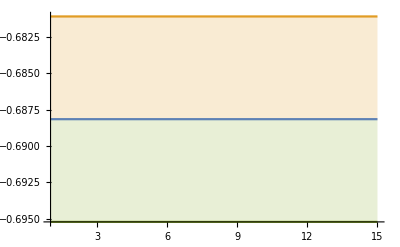

```mathematica
Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,15},Filling->{3->{1},2->{1}}]
```

```mathematica
SpoilHWFLOPlotN3=Show[Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,Length[meanErr2[[5]]]},Filling->{3->{1},2->{1}},PlotRange->{-1,0}],ListPlot[{Table[{τSteps[[1,i]],meanErr2[[1,i]]},{i,1,Length[meanErr2[[1]]]}],Table[{τSteps[[2,i]],meanErr2[[2,i]]},{i,1,Length[meanErr2[[2]]]}],Table[{τSteps[[3,i]],meanErr2[[3,i]]},{i,1,Length[meanErr2[[3]]]}],Table[{τSteps[[4,i]],meanErr2[[4,i]]},{i,1,Length[meanErr2[[4]]]}],Table[{τSteps[[5,i]],meanErr2[[5,i]]},{i,1,Length[meanErr2[[5]]]}]},PlotRange->{-.1,-0.005},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]],markerlist[[4]],markerlist[[5]]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]},PlotStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau_{\\text{steps}}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3(\\text{NNLO})",Magnification->1.2]]
```

-Graphics-

### a=0.8 dτ=0.2

#### QCD LO - HWF

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={430,430,430,430,430};
NWalkers=200;
Nf4α1LoopBig={0.8,0.8,0.8,0.8,0.8};
aList={1,2,3,4,5};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
csvData=Table[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"],{xx,1,Length[aList]}]
```

({mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.07596541373089014, -0.07591961547197891, -0.07581978963168441, -0.07594101777237273, -0.0759034194747049, -0.07586643294012221, -0.07595056613482741, -0.07605122286451758, -0.07600551295727803, -0.07587994150802557, -0.07593590911842746, -0.07589000315076821, -0.07582793916358664, -0.07591420236579945, -0.07589198800865421, -0.0758788284792071, -0.07592833293510026, -0.07588851854462249, -0.07597458831757795, -0.07605392361295728, -0.07599859716619194, -0.0759271523766691, -0.0759828828252292, -0.07601219311512393, -0.07596271468920142, -0.07606363603866541, -0.07622489489360751, -0.0763429866092387, -0.07624662532583333, -0.07608586063980928, -0.0761659326772016, -0.07615492787223747, -0.07610495468114604, -0.07604938135056366, -0.07603686972985244, -0.07599375903288183, -0.07588140014647832, -0.07587334378093032, -0.07588102927373322, -0.07593107459382871, -0.07601044464242485, -0.07604658831189277, -0.0760387626656112, -0.07591912335622203, -0.07599446268129965, -0.07589027009253178, -0.07597005947225348, -0.07592859045080863, -0.07580957744600841, -0.0758113224314644, -0.07579015491118857, -0.07579527026492246, -0.07581673247542822, -0.07596207796028559, -0.07585519543274596, -0.07577981005186905, -0.07584969599866921, -0.07582198614624937, -0.07591323049273561, -0.07587491810217607, -0.07597288245512328, -0.0761328354266402, -0.07612220572721796, -0.07605584655686486, -0.0761423639752737, -0.07614222554761764, -0.07615191190286866, -0.07615238606864, -0.07622490122588914, -0.07624479349642996, -0.07628834881413138, -0.0762750469737819, -0.07626501601862176, -0.0762693139221733, -0.07625845784925446, -0.07630656599092842, -0.0763478181169777, -0.07625287712844105, -0.07619860524108614, -0.07611561722202348, -0.07608529266963679, -0.07600285086019429, -0.07599994617238053, -0.07587377497287892, -0.0760257441102825, -0.07610586485402904, -0.07628215939627866, -0.07625731419485389, -0.07622893085966258, -0.07624552212792716, -0.07620169707838984, -0.07623988297673401, -0.07620741214308556, -0.07608070665188706, -0.0760361814647469, -0.07603935902661797, -0.07600102480084897, -0.07606066840769851, -0.07610836797013258, -0.07613202326946991, -0.07604020637668485, -0.0759674982262111, -0.07591981740093648, -0.07591808074313851, -0.07589206212191796, -0.07598767075002061, -0.07619642860775108, -0.07609965786387732, -0.07608229017441302, -0.0761953151420809, -0.07602412866552467, -0.07626955166114947, -0.07629328813589419, -0.07622434904893931, -0.07621045144290989, -0.07622977856219208, -0.07618074336629733, -0.07629044489107398, -0.07613473554385365, -0.0763112981121015, -0.07629784518174978, -0.07634650400283441, -0.07633220768310424, -0.07631651440735232, -0.07621537809953928, -0.07631223640664257, -0.07639105180110509, -0.07626683408543655, -0.07640872895812846, -0.0764301019908393, -0.07638292797265757, -0.07625998959062506, -0.07627439191780173, -0.07633823155865709, -0.07636746152502082, -0.07629348910461645, -0.0763431191814842, -0.07636720328363393, -0.07617682054161427, -0.07602913440107369, -0.07595005419428942, -0.07600843192564187, -0.07619502713583334, -0.07632930739301731, -0.07630751884828438, -0.07611349286716138, -0.07604080766121067, -0.07609144678469251, -0.07610690105374779, -0.07604668608790423, -0.07605769080907496, -0.07611139097721566, -0.07603242353378672, -0.07603080409750566, -0.07589915823565539, -0.07579141745717008, -0.07573669365907522, -0.07564655702030587, -0.07588434978899244, -0.0759866167548628, -0.07595829928036045, -0.07578247681190968, -0.07579746811871259, -0.07577002195565254, -0.07596005684121024, -0.07606184508320002, -0.07606189549727857, -0.07606992736021033, -0.07604025587877035, -0.07606770979086405, -0.07606712338811543, -0.07609772019309798, -0.07619201942976435, -0.07607158504659894, -0.07604238515364525, -0.07591253762996987, -0.07604166264368868, -0.07624036285066006, -0.07628711549484207, -0.07617859563097314, -0.0762834484720083, -0.07630311466890763, -0.07628858919422266, -0.07635184955472911, -0.07634756802698439, -0.07617890980075533, -0.07635358351780056, -0.07627108754391586, -0.07628957633273983, -0.07645783146101752, -0.0764444344591897, -0.07625627672576786, -0.0761384116901619, -0.07620836379213448, -0.07606793562826808, -0.07622865702095762, -0.07624887680989095, -0.07604018500306446, -0.07605090481582961, -0.07621090775403812, -0.07635655654530903, -0.0764008954783349, -0.07635467035488314, -0.07630632217503995, -0.07622864677667453, -0.07628762369991812, -0.07633515505511981, -0.07633028099977007, -0.07621706910598029, -0.07627914838987523, -0.07611786649209017, -0.0760670853277089, -0.07624195658267004, -0.07613701954205693, -0.07634296158702818, -0.07633446407048071, -0.07627199443761258],[0.00018688026201120063, 0.0001891219610088073, 0.00019620933478006926, 0.00019746812566637234, 0.00019771878423334823, 0.00018828016747839482, 0.00018908242889033766, 0.00018603676498088405, 0.0001841095892752252, 0.00018877406920575382, 0.00019535291334310108, 0.00020040233487456124, 0.00020571590328442562, 0.00019596257870965492, 0.0002139577218398531, 0.0002073832180479653, 0.00018993995611970934, 0.00019454083969852284, 0.0001933698928994644, 0.00018655143470780767, 0.00018680521118280547, 0.0001783243729526186, 0.00017456220304598054, 0.00018510957930061952, 0.00016906085328127418, 0.00017362492820141093, 0.00017598897303102787, 0.00016137613371167983, 0.0001571417903236154, 0.00016434737092805207, 0.00017879306017451674, 0.00017899053869526485, 0.00017957815063768663, 0.0001797487386075519, 0.00017944977350351236, 0.00017926114098607072, 0.00017306638358720257, 0.0001755462592871505, 0.00018176447375436305, 0.00017280205687995466, 0.000198992030366274, 0.00018464466900442995, 0.0001955556560971391, 0.00020644209934195248, 0.00020609197879574865, 0.00020110532216605835, 0.00021304825822445614, 0.00020970433816995068, 0.00020354751878740973, 0.0002052798502243241, 0.00018173830366749396, 0.00018104175362885944, 0.00017172311204919892, 0.00016779590917104136, 0.00015782534865717486, 0.00016240976665093403, 0.000159578016728706, 0.00015896903831682762, 0.0001586503268927292, 0.00016377748651507837, 0.00016081675131439455, 0.00016316142524373922, 0.00016423707605352114, 0.00015434075076593384, 0.0001749264764455802, 0.00017109725698316166, 0.0001741586311084966, 0.00017668395673047367, 0.0001823377231747293, 0.00017733640392491885, 0.00019158193118613723, 0.00018847372411664393, 0.0001914551416890421, 0.00020661734063559604, 0.00020480018404727494, 0.00019872477812786813, 0.000188706860894749, 0.00020051696838142673, 0.00019828671386486318, 0.00020404289383114095, 0.00019633538209232288, 0.00021311479045337664, 0.00021221422889363564, 0.00022491618636485803, 0.00024673618606308644, 0.0002683079186139095, 0.00022964629804732788, 0.0002338465355437824, 0.00022311428060152076, 0.00021520173510712617, 0.00022599811000895538, 0.00021804521231129505, 0.00023172540098666136, 0.00023137726493094586, 0.00020945229412036335, 0.00021425372929671804, 0.00021806225165167925, 0.00020438838192201288, 0.0002004910752676732, 0.00020243837375058293, 0.00020725100146376903, 0.0002149888166406244, 0.0002100163289922004, 0.00020257867761186562, 0.00019683332642049522, 0.00018685401704049133, 0.00018123575571784556, 0.0001961937290085094, 0.00020973035606542187, 0.00017937883153424804, 0.0001894460620810457, 0.0001930551544321137, 0.00021013161933070094, 0.00020567328013726397, 0.0002179444421879253, 0.0001920796666470539, 0.00018282078866168683, 0.0001782902465908473, 0.00017018299637857733, 0.00018761299926665535, 0.00018373574458634373, 0.0001765776502819943, 0.00018115995706825312, 0.00019961680382708937, 0.00020520249810337263, 0.00019909649617991904, 0.00020028459912088478, 0.000187185871794503, 0.0001993738936275228, 0.00022327571461188528, 0.0002014051707626137, 0.0002158783034622225, 0.00021140091587672325, 0.00019857923857339528, 0.00020545813334888074, 0.00020261720589956635, 0.00020842119501932282, 0.00021745527969674916, 0.0002311426169325868, 0.00022850322108549815, 0.00022895661791051585, 0.00022691625736060624, 0.00023111825934247652, 0.00022255733506185488, 0.00022011365117284747, 0.00024801173079842424, 0.00025380842204953676, 0.00023566111526289658, 0.00022463452937200218, 0.0002165863392676856, 0.00020667641658321528, 0.0002175785643700745, 0.0002173807391650935, 0.00019964029333929776, 0.00020112198720469444, 0.00021196848723010513, 0.00022453767634203535, 0.00021307217702617705, 0.00019675786749454933, 0.0001907664823355592, 0.00019235230007987874, 0.0002066137310417952, 0.00020313092905206286, 0.00020775997614251482, 0.00021670785435580004, 0.0002103950759421865, 0.00020240063060021892, 0.00019457009957492342, 0.00019309388935078052, 0.00018097970106708427, 0.0002165324445333748, 0.00020283250113876795, 0.00020319648223425537, 0.00020591355100760443, 0.00020495476593794962, 0.0002050277501234565, 0.00020467345575791963, 0.0002011714340169579, 0.00020904843782261124, 0.00021190999251254078, 0.00021709058596169775, 0.0002083494446831342, 0.00021401347636835474, 0.0002016111014028046, 0.0002013931074000366, 0.00020934717784044417, 0.00019560819451202823, 0.00020103127379974303, 0.00019906927212808655, 0.00021179208000523717, 0.0002149834017458492, 0.0002309276885794538, 0.00020984548623897205, 0.0002132289263108225, 0.00021584407172062852, 0.00023233562031991188, 0.00024042610199584037, 0.00023112809707211268, 0.00022154969850158752, 0.00020703158422502807, 0.00020966157186431264, 0.00021573339137155546, 0.00021478331215940119, 0.00022482409246895167, 0.00023729911637003842, 0.00022210097874299413, 0.0002235680927254417, 0.00021733439159436538, 0.00019989860149438916, 0.00020046959428901394, 0.0002065218827281602, 0.00021150165026407596, 0.00020145854027660775, 0.0002048196709280187, 0.00022472757226220662, 0.00022960153551586604, 0.00021863242545863047],-0.0761121,0.0000347226,2.38103}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.056974006153863874, -0.056775384051905846, -0.057593163867654645, -0.059053340783944225, -0.06020803290566647, -0.05918887313388613, -0.059463335680710064, -0.058723357459605934, -0.058219655486268576, -0.05677536983497551, -0.056515751766161984, -0.05651201520497978, -0.05622433213704227, -0.05659381853922874, -0.056233486004643965, -0.05648034578916046, -0.056722087267607406, -0.056991131128382354, -0.05734089299674825, -0.05831471491984427, -0.0574797624045109, -0.05773422046270046, -0.05854890000409694, -0.05879959859118027, -0.05787560839538194, -0.06006643859330224, -0.059078209330864245, -0.05915838907860894, -0.05764909207510685, -0.057628086915865906, -0.0571038639442474, -0.05698667673032746, -0.05696385188928453, -0.05712409870205039, -0.05835266430282213, -0.057803896790819924, -0.05809011217849075, -0.057498029741060296, -0.05858808875237572, -0.05870309278613788, -0.059783848605758486, -0.05894588155243827, -0.05855292299757448, -0.05852592286854205, -0.05883365047391066, -0.05917919124968299, -0.05874560503530919, -0.05916322895453911, -0.061156673849146546, -0.05945436559745296, -0.061307817126817446, -0.06068324604338942, -0.07022058306342116, -0.06616764841533546, -0.0634447776115575, -0.06224800941950284, -0.06284422492514949, -0.06604695394155678, -0.06300122310704752, -0.06067803081001702, -0.06030332728703759, -0.061774215862907246, -0.060749002951386334, -0.058717606975852196, -0.05939457420532998, -0.058875360547205706, -0.061565766420972445, -0.06376295576350448, -0.06095859850458591, -0.06133208474650194, -0.05859749152962947, -0.05959203144994072, -0.05769427638199498, -0.057579435248467585, -0.05753658280550652, -0.0572828257899547, -0.056594184984529554, -0.056833176350079444, -0.05672981093020991, -0.057386807764174444, -0.057375199569086884, -0.0571036645841784, -0.05701560078392285, -0.0570611710516387, -0.0569737836879105, -0.0572579131108663, -0.058081905038426966, -0.05825277485441634, -0.057568114869010464, -0.05851473898359967, -0.05857439994699238, -0.05839450026862336, -0.05890842808408043, -0.05910354132435264, -0.05855140864755814, -0.059032804770524624, -0.05841437745373857, -0.05826714844748833, -0.05926302107773842, -0.059440240564668685, -0.060532044799386994, -0.06137410789693414, -0.061151147766768554, -0.06352908757056222, -0.06036212191140712, -0.05925379253350495, -0.059488579252122226, -0.059365328033743454, -0.06049764713352402, -0.06027318058700643, -0.060368531429829564, -0.05965643792417664, -0.059568702737852766, -0.06348672687015286, -0.058379292066265596, -0.05803078972581784, -0.058909158307600344, -0.059462689742517866, -0.05834998118226004, -0.0582547095856578, -0.05899436952323471, -0.05866969493712188, -0.058720733043772844, -0.05964882682198486, -0.05931434079517464, -0.058767198200989655, -0.057861215993424336, -0.05916058411754282, -0.05961560956399129, -0.058578194063786705, -0.05827767093639962, -0.058648345662292295, -0.058592587851171704, -0.0588951249543359, -0.059740299438516546, -0.06058401766069235, -0.059609701711690354, -0.05972163066290145, -0.05992403350552558, -0.06005236908864344, -0.05966011426299766, -0.059820532702353976, -0.05966499649821446, -0.06101268571182885, -0.0606856027735887, -0.061400283641886974, -0.06097503439428445, -0.062354030467254, -0.06141035111337511, -0.06182281498331873, -0.06261486598440931, -0.06187142771432764, -0.060865462291241505, -0.06048080208276365, -0.061218700341649626, -0.061071125612349134, -0.06139606497062329, -0.07847571207926558, -0.06223111974322468, -0.06261602784102743, -0.06301885091871132, -0.06321245147834928, -0.06216653248996035, -0.06148950616253717, -0.06338095160621096, -0.06816258121804379, -0.06318761864206807, -0.06402422492609118, -0.06408222977216282, -0.0642170206003495, -0.06582956755912679, -0.06883723935635523, -0.06805646617071419, -0.0695885843380686, -0.06755776025434924, -0.07047067810756603, -0.06721522979464972, -0.06902339021791135, -0.06735000190500554, -0.06575447460657348, -0.06636715383391474, -0.06571343409501909, -0.06673017426664057, -0.06666260983008265, -0.06616265116581849, -0.06645519882263637, -0.06774599450575758, -0.06687450284517184, -0.07070116823947714, -0.06825115671852405, -0.06643363805064559, -0.06668511571038988, -0.06595376442424278, -0.06819674415916106, -0.06922171202390773, -0.06926610338414196, -0.067885353431062, -0.06804542340191945, -0.0681705101868988, -0.06830254072761235, -0.06861066939582561, -0.06793272069836905, -0.06820564016170462, -0.06728289823986439, -0.06732326954856493, -0.0673486274268228, -0.06795929141024878, -0.06870351047410311, -0.06836846010571465, -0.06915761224323946, -0.07138828238646144, -0.07320910705981958, -0.07064616968051067, -0.07150936598097601, -0.0736335917622122, -0.07113048450531742, -0.06913322742113528, -0.069365253501277, -0.06795473710466775, -0.06911572712458378, -0.06839383507137663, -0.0691498635005977, -0.06906696093375275, -0.06963179095628669, -0.06981865055002848, -0.06968401427065743, -0.06918758908563533, -0.06906110418653578, -0.06766998998475857, -0.06829518883331674, -0.07008451545991602, -0.06926634845623329, -0.07382120980080084, -0.07695607295661351, -0.07290972298070655, -0.06810365793453073, -0.06867391611824006, -0.07267113510525475, -0.06736232226097248, -0.06664147378345085, -0.06676278555622342, -0.06763764272336754, -0.06732272620422397, -0.0680767801079977, -0.06741086089841565, -0.06848577178635572, -0.0679431170945941, -0.0662060567118225, -0.06585574407817261, -0.06724973539034468, -0.06834219182664365, -0.06731694522036885, -0.07157448844786117, -0.07807120256011499, -0.07427758015889667, -0.0755668210507586, -0.07243836465737519, -0.08523799495084017, -0.07629093440109964, -0.07094853791128906, -0.07010355495080195, -0.07058732632075157, -0.07464842528999581, -0.07287389550033897, -0.07280333709480691, -0.06930944536923685, -0.06930647044838469, -0.06824136251917912, -0.07032963705240176, -0.06816978308052918, -0.06901753526413684, -0.06889716810589973, -0.06831752555807008, -0.06703566613303594, -0.06710974077385527, -0.0670928133278064, -0.06681331381093751, -0.06669778719764383, -0.06627429346815089, -0.06625514015768583, -0.06754007093148585, -0.06998057716800678, -0.08494441254397136, -0.07466563629565115, -0.07365161871040718, -0.06973252070100897, -0.07140965310006504, -0.06934313730820157, -0.06747954385530265, -0.06676575787655106, -0.06613749521638208, -0.0655589303838165, -0.06544007650766412, -0.06492585331764257, -0.06581146339872766, -0.0665113936430973, -0.06574978562737166, -0.06601555955891412, -0.06526587871128227, -0.06450855807581511, -0.06475338410388788, -0.06583168934051191, -0.06517897754488179, -0.06553448862078953, -0.06467981176782708, -0.06724012540382153, -0.06969806698314061, -0.06826581741857335, -0.06827933563605632, -0.07343546802004611, -0.0704222924296187, -0.07604700241602134, -0.06749048049521703, -0.06644670479014184, -0.0673043274571289, -0.06660492890477013, -0.06563646390631354, -0.06595172948450122, -0.06534585153867313, -0.06637098795671544, -0.07043869390606923, -0.07325201473195607, -0.06499817315387652, -0.07011887388032167, -0.06935574446612347, -0.06736689764401665, -0.07028324173289943, -0.06673749376781203, -0.06721644355072853, -0.06642780240074202, -0.06793945731992014, -0.06681776966424616, -0.06829878975987645, -0.06845212233163812, -0.07099586328918724, -0.07022032971537641, -0.0677186857333318, -0.06671795701351863, -0.06645023794343885, -0.07292810987603887, -0.0676581825343183, -0.09811417053379094, -0.07018983467898926, -0.06944026846403702, -0.06692826077540333, -0.06590501200931868, -0.06545155557457162, -0.06536805331542628, -0.06629058323174376, -0.06565077567594345, -0.0666263666131523, -0.06783423622209311, -0.06839757924689654, -0.07044425583552417, -0.06954807437145621, -0.06861465390901503, -0.0696995619628048, -0.06992972246683526, -0.06906370090742099, -0.07163756097673382, -0.07049361309813726, -0.07128189068227901, -0.07071172716400555, -0.0715663497333192, -0.07084781097129754, -0.07007096870837831, -0.07096988955763156, -0.07083069789794696, -0.07346071664223293, -0.07114707294885309, -0.06967795484386372, -0.06880957848878724, -0.07011945727814962, -0.0700798424043549, -0.07276387571097018, -0.07052844207689468, -0.06931690254256917, -0.06926816115572344, -0.07034532175472406, -0.07171777136447392, -0.07232910511035859, -0.07356722704894629, -0.07265376503939378, -0.07139498041282501, -0.0739866478507897, -0.07314840367254327, -0.07474929564838591],[0.0012829873706722383, 0.0012989365305518137, 0.0015984035778738954, 0.002044873550145068, 0.00240149533893118, 0.0020211754929269194, 0.001978183329408273, 0.0017568526605776103, 0.0016014187189812192, 0.001301825918005332, 0.0012116791228307955, 0.001178192050772632, 0.0011237103222061615, 0.0012049174570046414, 0.0011662910642679819, 0.0012444281462057082, 0.0012664329953144455, 0.0013436745725497977, 0.0014338160087299188, 0.0017609210913185013, 0.0014143632744465513, 0.0014865000220669632, 0.0019499602587445821, 0.0020322819830934195, 0.001705692288866745, 0.002978359136987281, 0.00219912452817932, 0.0023737116062084234, 0.001635155006059453, 0.0015890351591221537, 0.0014171006798506846, 0.0014203836998171807, 0.0014681112510388599, 0.0014862300644552205, 0.001849064515811285, 0.0016854655029772665, 0.0018011191088305768, 0.0017298044641510168, 0.0022011170957383017, 0.002213808557629005, 0.0031473408662489946, 0.0025377909322134382, 0.0023360312664691156, 0.002310436218493982, 0.0024273346263840997, 0.002822207149634219, 0.0025376976032564225, 0.0024237587687202648, 0.004521670473284499, 0.0032242927550128267, 0.005133027661033696, 0.004436589659229103, 0.014485510112061019, 0.009910458201352562, 0.006473648053684121, 0.005483911432652311, 0.006124082599849166, 0.00915695760933968, 0.005779536049082377, 0.004267240483697186, 0.0042738896096565955, 0.005696002493201319, 0.004401548759393395, 0.0030283336823307013, 0.0033649874567075735, 0.003490954555398316, 0.0055140956363219674, 0.007591961109286058, 0.005037320409343654, 0.005485811340069825, 0.0030491453036706096, 0.003201725094352188, 0.002083542419539453, 0.00200679994351294, 0.002034569451851914, 0.001896655298282198, 0.0015134786180720317, 0.001700163828582605, 0.0017263865057732205, 0.002044761892716094, 0.0021620010420168, 0.001870449095890484, 0.0020145320033453625, 0.002027644568660814, 0.0023684760208511533, 0.0024786801735921767, 0.002742119728498172, 0.002915724117739626, 0.002439583287020646, 0.0029949848184805503, 0.0029117917192495665, 0.002682205501313932, 0.0026070834333468303, 0.0026004320347344312, 0.002422262091476933, 0.0024265188420216463, 0.0022706726589022163, 0.002132982533143929, 0.00252477230936116, 0.0027956196811882755, 0.003457047015969107, 0.0032857339815224253, 0.003379859687297506, 0.004818442096526374, 0.002779260441082472, 0.002236720869249664, 0.002229416195508304, 0.002079796952885801, 0.002420285818495462, 0.002325615846838394, 0.002364113152456317, 0.0020996467429891773, 0.0022663506472739695, 0.0063915041263330925, 0.0017926544244167555, 0.0016594214596286694, 0.0020003425995621924, 0.0022654579086323207, 0.001656782993596044, 0.001593548751178805, 0.0017364334142477486, 0.0015847892464374105, 0.0016397037393811988, 0.001978818501706707, 0.0020411971449538387, 0.002097232854073705, 0.0019610594312212595, 0.0022582089267598657, 0.0023546345165311763, 0.0018451533433621198, 0.0015516061211094249, 0.0015977655432843328, 0.0015498613631187703, 0.001588829287587836, 0.001794205806729952, 0.002011747787690901, 0.0014151700050798071, 0.0017558819696640836, 0.0023635139579416702, 0.0023294745034312197, 0.0017269523515460405, 0.0016151317404123186, 0.0014453329108593679, 0.0017780757707241556, 0.0016823373447462967, 0.0018582984335384748, 0.0018265363246435932, 0.002302840827760262, 0.001703784463154622, 0.0017406120233064845, 0.0022718835444879813, 0.001956789361913724, 0.0016443741499482655, 0.0014821043072904619, 0.0016235752917446633, 0.0016828156159515864, 0.001698683792976526, 0.01697044402319223, 0.0021224237939477973, 0.0021484522295327456, 0.00235986991120967, 0.002605794771274175, 0.0018134031621232808, 0.0017667721164291302, 0.0025441279299187065, 0.006128394992040049, 0.0024549323929459466, 0.002536827351310886, 0.0025941674404854438, 0.002499017903372452, 0.003379062210125778, 0.004510864378738295, 0.0035797511149486473, 0.004193903631789702, 0.0031865650107510534, 0.003935261277327046, 0.0032721463063340762, 0.004620936458355249, 0.0030464403349837192, 0.0023303695908739722, 0.002494051478070221, 0.0020953305697345697, 0.002319283673285259, 0.0023709726235731166, 0.0024441871450632297, 0.0023328905646404874, 0.0026420051189349866, 0.0025733041323181645, 0.005112644713430903, 0.0033486719778189162, 0.0027102055734533545, 0.002699297695461491, 0.002393622815400136, 0.0035634820894414154, 0.0038089082816649524, 0.004009708059019358, 0.003872376070136103, 0.0039453332568674905, 0.004234924129865995, 0.0036522299369993465, 0.0036169731362103922, 0.0030721771592802623, 0.003383722364235486, 0.002572351663128292, 0.002789863363572304, 0.002563595036467167, 0.0026493917168863624, 0.0028390050198045594, 0.0027406237034246707, 0.004322955449731848, 0.00563062011301121, 0.006719716221990897, 0.003610747438173328, 0.0041132646823286104, 0.004668932104925027, 0.003184706141731273, 0.00266349239258884, 0.0027971545331021965, 0.002233261621182066, 0.002403733686272988, 0.0022996764342334023, 0.002402768900590501, 0.0023580595655058414, 0.002673396930700566, 0.002720437343416466, 0.0027483418041967587, 0.0027151612593064468, 0.00256893765666928, 0.0022915018056512406, 0.0028257275483560976, 0.0032081556728403068, 0.002912661772245, 0.005346126316836667, 0.008416705200919888, 0.005129820770926728, 0.003166965992251535, 0.0035172884158169806, 0.00677675742925352, 0.003105941223450146, 0.0026645977048228237, 0.0029224675845090317, 0.0037790811082507574, 0.003326284563729245, 0.0036391103151451414, 0.003571544328439652, 0.004147320045388078, 0.0033635760850288777, 0.0026345368190698265, 0.002760490415928719, 0.003250529602617758, 0.004526140765906207, 0.003038105469917825, 0.00537766659751547, 0.011389899185978844, 0.007918718790289941, 0.00854500731181283, 0.007199703823549282, 0.016919778839329467, 0.009373480756484448, 0.00501634228458133, 0.00456414342634558, 0.0045529488717595675, 0.006736360271600709, 0.005339344450834313, 0.006453878462231157, 0.0035690763386912994, 0.004363092865036191, 0.003858721099571001, 0.006082030275644714, 0.004326872823724183, 0.004782872478975377, 0.0044797070174455245, 0.0040505022666371395, 0.0032353854327458876, 0.003134102304850928, 0.002789586483323889, 0.0027241782314262495, 0.0027939604665116195, 0.0030376998932012816, 0.0029600486847446606, 0.0038310199450636933, 0.005786110236171987, 0.018538017775027366, 0.010093471716686774, 0.009623845012798275, 0.006428766608551453, 0.007560506867505958, 0.0054010706568788334, 0.003584677805499499, 0.00336085185901539, 0.0029689727493890615, 0.002933155809724273, 0.0027889679958802284, 0.0026066816641978972, 0.002910510607760061, 0.0033943641212864405, 0.002943279569098429, 0.002845127515185762, 0.0027456221773522562, 0.002221417030472219, 0.002287473481872675, 0.0027200689241147612, 0.0024252529902409085, 0.002241121262404206, 0.0019138382348474526, 0.002857567804061164, 0.004363489236270105, 0.003914682454457886, 0.003964332525164858, 0.008305355368573776, 0.005473422257381692, 0.011657126854323682, 0.0027805719164551343, 0.0026106100405962444, 0.0031001472434774606, 0.0028154079919540604, 0.0023169390112370183, 0.0022712713620466, 0.0022222535087598537, 0.0030858675470132944, 0.005363807905024882, 0.007643456384516074, 0.0022821450573360705, 0.004956545273516601, 0.0037735893892499933, 0.0029465761440435555, 0.004964057628257758, 0.0023958769905450617, 0.0026208990642856184, 0.0023596851603710205, 0.0031282931456466444, 0.002464014155127506, 0.0034082792405789437, 0.003281894971384955, 0.005178502659522288, 0.003977458850055467, 0.0029111389464262245, 0.0027984256753345016, 0.0028066067592387657, 0.007279376828584036, 0.003424631296126286, 0.033421475268349994, 0.005736402287298546, 0.004573785904742693, 0.0033760555819191867, 0.0030644479844880645, 0.00283453376955369, 0.002670213186930073, 0.003014028538981992, 0.0029505499883202566, 0.0033114334532104044, 0.003879530292004219, 0.004059648342515447, 0.005209622053510183, 0.004372420853996512, 0.0037427206971138985, 0.004258757289354458, 0.0044575014087968445, 0.004288556285998401, 0.005377247275538037, 0.004653752450125202, 0.004947024618030232, 0.004901715400664472, 0.00553583119440978, 0.005101410333998104, 0.004255162060628832, 0.005014895887461533, 0.0054095822748455894, 0.006931345499989449, 0.0055011937029917825, 0.004359215681849875, 0.00393232338638509, 0.003972861428074488, 0.004062702249281475, 0.005228916454759909, 0.0035524425412913137, 0.002962968899288282, 0.002840201688362141, 0.003190608697751311, 0.003457376285279681, 0.003779746775717651, 0.004384410573722007, 0.004302808703602423, 0.003987890946154092, 0.00475760803042045, 0.004571665721768606, 0.004826564189798201],-0.0580098,0.000477414,0.502067}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.045612558888762894, -0.04560917657072649, -0.04486279722826777, -0.045447014389643076, -0.04583861648368492, -0.046558548193253425, -0.04597911131447267, -0.04577644703815697, -0.04697493239871723, -0.04560756099307158, -0.04470820081464392, -0.04532649582722837, -0.04539277571628667, -0.04611338823681879, -0.04569724519892796, -0.045793350751722056, -0.04614126701099321, -0.04590072106647264, -0.046105825725481824, -0.04750552120888664, -0.04703027620268904, -0.049292799873632415, -0.04728088634552355, -0.047464148631404406, -0.04690247314901137, -0.04599109139068944, -0.04708682558054064, -0.04646580986327204, -0.04714076866179592, -0.046131785364563284, -0.04692321660700277, -0.04592679692562311, -0.04573635083741819, -0.045094877589990465, -0.04623012085345234, -0.044469434512078874, -0.04478036962297486, -0.04446682803434125, -0.044542370299570394, -0.04436346146032874, -0.04419584714050411, -0.04394330202044391, -0.0441811366596703, -0.04403438166057667, -0.04393192700293412, -0.04382934447107872, -0.04405297774092949, -0.044417023528456584, -0.04406517477735229, -0.04385405339876704, -0.04367459715232789, -0.04348981223988353, -0.04312235410480322, -0.0433696168873682, -0.043517590451712385, -0.04355111752501519, -0.04364508938902887, -0.04376910646973328, -0.04409101152086982, -0.04385355779687085, -0.04403899595873457, -0.04370005895961564, -0.04380338950731869, -0.04357773634868937, -0.04353726533056552, -0.04357220308434893, -0.04399407049272535, -0.044177332049909965, -0.04486212842579987, -0.045226085300725805, -0.04530792206655342, -0.04685807843529935, -0.04677931641009516, -0.04566414220012048, -0.045984607114592256, -0.04569905182409844, -0.04643474227183254, -0.04609103817680242, -0.04556628979857121, -0.04652159395108596, -0.046648120295435865, -0.0457747134807421, -0.045406492218954965, -0.045590359571999944, -0.045812077286666086, -0.04615858302192427, -0.046647078840354746, -0.046494693914416185, -0.04642451336848303, -0.04657954202951411, -0.04758502151828695, -0.04734991895247465, -0.04663656560161996, -0.04693244248918746, -0.04700170591754242, -0.04703367281894781, -0.046216349532557544, -0.04669610134493025, -0.04686541682210722, -0.04713022351941272, -0.04712520730235564, -0.04742865396625001, -0.04696750416765594, -0.04707261896380689, -0.04675488412277739, -0.046930225363355775, -0.0474872438543503, -0.04678884076216782, -0.046822069848817024, -0.0471707273233102, -0.047458725530207344, -0.047782488285627686, -0.04956563782344539, -0.047954074997044585, -0.04914833291038496, -0.04862438310898013, -0.04987079058884602, -0.049215275187204865, -0.04991545695425749, -0.04933827021820708, -0.049469671438385786, -0.048465332953980624, -0.04756097535847679, -0.047293562739120325, -0.04709114919410773, -0.04649036865978689, -0.04638571424104016, -0.04701228177592493, -0.04721305854392882, -0.04718644342669414, -0.04740995617922706, -0.04846639731123415, -0.05051210229062359, -0.04788096477396084, -0.0497596580293143, -0.05030016016929114, -0.051915451941459835, -0.04838215519853848, -0.047640489618909106, -0.04771024647167507, -0.04967336414653784, -0.04882481112478744, -0.04823128681057897, -0.0482876124982893, -0.048590312412855795, -0.04930781398406621, -0.04812495372159232, -0.0495371493084768, -0.05139807931392534, -0.0509402126426473, -0.04913187214499297, -0.05017603568972383, -0.05310229772660007, -0.049903137207019214, -0.05057244774286215, -0.05173945878408293, -0.0510614543186007, -0.050889672280654705, -0.05141022244381792, -0.056366250068605635, -0.05200482574321912, -0.05305915945627796, -0.05331830237254759, -0.05276530355120823, -0.05379527536431321, -0.053138767913912685, -0.05214145053653489, -0.052632983493727595, -0.05244554463845786, -0.05276801762103268, -0.053415038010626165, -0.05462647459384543, -0.053029124385149215, -0.0532057951039009, -0.055782270776250586, -0.05425610059832395, -0.05415170785217523, -0.0535173233855734, -0.05350866578538371, -0.05914023750299016, -0.055145398373838125, -0.05524832797814255, -0.05293950865276763, -0.05323885080867222, -0.05378864636249396, -0.053726888439065305, -0.055446483717126384, -0.054120883152568695, -0.05488122228385444, -0.05468297142266402, -0.05415845899854713, -0.05408213379181174, -0.053090460095743544, -0.054341423690698706, -0.05576976229389953, -0.05661596828185969, -0.0577794023067, -0.05604769770817783, -0.057566494653709235, -0.059860214642865395, -0.06010431075333302, -0.0556227534712569, -0.057054172363442714, -0.05737012658341667, -0.0543318694573831, -0.055170069426604525, -0.05529666128138053, -0.05546770008458589, -0.055351554730643654, -0.054725456061868065, -0.05412232482817846, -0.054790389362977004, -0.05465800880986633, -0.05490261215787294, -0.05521478144460555, -0.055371546070608735, -0.05486565518343426, -0.05805710760699417, -0.0627172239538822, -0.06692428946720229, -0.06412049677024083, -0.0648872425818413, -0.07396752685095642, -0.06398036093556723, -0.06544673197673379, -0.062335717302009076, -0.06017817283353703, -0.06082646427813083, -0.05906149408136097, -0.05907122792670423, -0.05998886523625088, -0.058809661073606884, -0.05868476437577854, -0.060733473753591095, -0.060904755901976755, -0.06410216379126936, -0.06500220666692268, -0.06876411737737444, -0.0654352212219085, -0.07534447235039571, -0.06732427679542109, -0.06447328635944752, -0.06359993521773614, -0.06412959157732458, -0.06522717432658966, -0.07237367568994155, -0.07909729817183099, -0.06688421981870812, -0.06395841376405383, -0.06495912434422678, -0.0643059934363471, -0.06344305198732543, -0.060987249558374354, -0.06684825086700535, -0.06755805211706423, -0.06376494165566167, -0.06442766264718726, -0.06801326415380121, -0.06164428519784523, -0.06028615706034184, -0.05790029101974863, -0.058556692384271865, -0.05774354330609653, -0.057902049819048666, -0.057904331193159124, -0.06077336778364674, -0.06044262219512535, -0.05849606714592082, -0.059698222154983986, -0.06243241146260714, -0.06344962357879669, -0.060885102237478776, -0.06169784067072247, -0.062296905931869095, -0.05972181922695936, -0.058398255403167586, -0.057917810121562815, -0.05849716827287754, -0.056339295278674394, -0.055884126610782514, -0.056157884018482734, -0.056406442333588235, -0.05628037340505564, -0.05675330466162458, -0.056971855812217156, -0.05649460116429214, -0.05571767592462022, -0.05495891760094451, -0.05513503960949359, -0.055038915168202626, -0.054592204124383314, -0.054448100868436426, -0.054454221727903755, -0.05419087616809347, -0.055044696808475686, -0.05556116754115622, -0.05448278385962741, -0.05540128305908178, -0.05410161524215206, -0.05285745801373535, -0.052995974934599926, -0.053610451872834045, -0.05397171313378036, -0.05594020398071097, -0.05478614887453909, -0.06552165918840892, -0.059622525824722564, -0.057622642041215553, -0.05721753672212781, -0.05515332613774428, -0.05474835064028918, -0.054009513560386545, -0.05405773491282293, -0.05320668988876972, -0.05291862136883886, -0.053645075616762586, -0.05395900828873818, -0.052883151493986626, -0.05216269017684964, -0.05112115995172785, -0.05149727040531452, -0.05116294369886449, -0.05234733053782713, -0.0526296172375708, -0.05301028735315363, -0.052811197499769556, -0.052689614092402956, -0.05278055618854402, -0.052889922922384265, -0.05383369019493742, -0.05429226866084038, -0.05354564574103169, -0.05516633017538543, -0.05823539998234251, -0.05820631564539554, -0.059961394108551946, -0.05848890419687765, -0.05892281115481779, -0.05831263270448438, -0.05962075497176574, -0.05834463404535379, -0.05761020383162954, -0.061499659828970106, -0.05959459416884442, -0.061005268192081887, -0.05906755931331962, -0.057039528156560215, -0.05716501738198277, -0.05773247590782718, -0.05781676674616003, -0.05795271942616684, -0.05832166736315032, -0.05928112676069098, -0.062461816341754225, -0.05997952570120059, -0.058882869329229225, -0.060697358239190834, -0.059049968821049376, -0.0588040448126416, -0.06021455343587351, -0.05986496634817596, -0.06062340644983501, -0.061056912711484744, -0.06444393354740613, -0.06549803001056526, -0.06889859210683107, -0.07472741026671544, -0.07071970967503781, -0.07240388072583316, -0.06877919801664181, -0.06470581334820087, -0.06251613006785733, -0.06522585976246237, -0.06423675937537239, -0.06288424472022902, -0.06615611606144645, -0.061628057385765656, -0.06308370196845477, -0.06507286584473489, -0.06331261691519538, -0.06850934793599235, -0.06599396495213115, -0.06604547842039529, -0.06487570202908935, -0.06952417249969069, -0.06980802875096943, -0.06733699658537798],[0.0018452961077714475, 0.001834547951826267, 0.0015876520329326858, 0.001752671449664693, 0.0019243284147615952, 0.0021246211877617616, 0.0018698301336468606, 0.0017503866512211363, 0.002448469607514918, 0.001965145022683856, 0.0015415020041634894, 0.0017756124249649096, 0.0018519945744379933, 0.002097783328199887, 0.0018940311638874364, 0.0018882460193359724, 0.002067936012622287, 0.001973708468667269, 0.00203049116477165, 0.0028948056498510877, 0.0024667759587516385, 0.003998751402550549, 0.0025510322223604074, 0.0027417510126858504, 0.0021959525629833077, 0.0018870794683797916, 0.0023340387484763517, 0.001881739998954618, 0.002523282169572421, 0.0018827996462979575, 0.0023085092569956915, 0.001784015490955169, 0.0017306514928532475, 0.001519182214777696, 0.0024868831044811556, 0.0012951471303141835, 0.0013259656820607563, 0.001290854875784186, 0.0013169456444832583, 0.0012928429775191503, 0.0013124756704152233, 0.0012441924001034036, 0.0013106327663361345, 0.0012685117504791315, 0.0012749464467901315, 0.001236559862775283, 0.0013070725302581317, 0.0013624144901177688, 0.0013619143774020483, 0.0013770507798420253, 0.001292254153025683, 0.0012224496914380624, 0.0012045557320087637, 0.0011737609657289602, 0.0012234907238313738, 0.0012128137358446457, 0.0011980186933510056, 0.0012003745443833803, 0.0012412508090528006, 0.0011780676921918623, 0.0012074003626675065, 0.001141113124829924, 0.0011714740667376853, 0.0011348542298257706, 0.0011348650170806007, 0.0011545065976372839, 0.0012016581601102683, 0.0012558337268421265, 0.001506890342699359, 0.0016300407303106023, 0.0018429188110021474, 0.0029834243654522684, 0.0025281152759039443, 0.0017276709413760942, 0.0017972895878368385, 0.001673209485843946, 0.0019649939919054843, 0.001777757724985107, 0.001665339755678943, 0.0018966167621266576, 0.0019243458927463957, 0.001672499423382096, 0.0015815364525319632, 0.0015658668492256299, 0.0016265413798001263, 0.0016968715680493421, 0.0017906953413041537, 0.0017759751865119326, 0.001793519902542567, 0.0018081908958235892, 0.0022921392409478033, 0.002167818950030122, 0.0019161133525573155, 0.0020325350474489703, 0.0019647792841184035, 0.002087930438022655, 0.0017869432919665796, 0.0018453297840369004, 0.001962798381155607, 0.0018907856840351287, 0.0019270312311149395, 0.002021058426606985, 0.0018797385685927846, 0.0018708172523689323, 0.0019238148763914243, 0.002152168729100023, 0.002452368533157879, 0.0021876486431991462, 0.0021081692143275297, 0.00236802681225052, 0.0024860087108625017, 0.0027932054882972655, 0.004451950528567992, 0.0028518110154704145, 0.0036796283746026565, 0.002827854072632094, 0.003571070766493609, 0.0029431574482301805, 0.0032106513192254444, 0.002981103475732781, 0.003142961995463977, 0.0028301903807989863, 0.0024013687144849084, 0.0023356134544703627, 0.002229602599194327, 0.0020772603504808874, 0.0019630229179119717, 0.002007028154855694, 0.002023841136745326, 0.0019224052597373272, 0.0019119384002924836, 0.0025815551030859384, 0.004056379435356956, 0.002134240184534818, 0.0030927619237811075, 0.00410903636912616, 0.00552161559668535, 0.0025693762067178095, 0.0019605754105346406, 0.002049215904791263, 0.002948939232893745, 0.002390964527209836, 0.0021951648792310333, 0.002017164202774203, 0.0021027124065326743, 0.0023960284815527227, 0.0019481648244000012, 0.002575580636712362, 0.003622615696311306, 0.0032830195926309516, 0.0021680110090570126, 0.0026878366593564764, 0.005228886071565349, 0.0025397320437289634, 0.002641359554010466, 0.003707548490247333, 0.0028685433409955494, 0.0025710157548976082, 0.0028080655468747163, 0.005520335816720001, 0.0031178901374417584, 0.003181372495887261, 0.003256559936627383, 0.0030986508929470163, 0.0031321547170508482, 0.0031010299032736438, 0.0026454414118500355, 0.002789138768030423, 0.0026193053768883753, 0.0026631259228038807, 0.003199064871980448, 0.0035458428521031706, 0.003069933087226326, 0.003029054075013807, 0.003974609259762329, 0.003153418361473503, 0.0031521225878794893, 0.002979041660109227, 0.0031722339130288205, 0.007048159657997956, 0.003531444256741918, 0.0038563073977371416, 0.002602395706916498, 0.002673314158025083, 0.00283809447845926, 0.002789970913484639, 0.0033191943314589073, 0.0029841916631108494, 0.003446300105565861, 0.003391535743595698, 0.0033967006334082537, 0.003470915221297047, 0.0030599337667241446, 0.0034540149564620945, 0.003857736558160241, 0.004273837383599196, 0.005070737085276075, 0.003952757702058964, 0.00522317767767958, 0.007050321845871849, 0.006942572102820757, 0.004102742046851622, 0.004844880122420096, 0.004711506694800947, 0.0031752781763617465, 0.0034743729849186136, 0.003419961228367, 0.0034463605884655674, 0.003378304426650945, 0.003049044671603493, 0.0028370690860712662, 0.003131069275070842, 0.0030631341646112356, 0.0032835199578354147, 0.0032067556380731715, 0.002950734898631854, 0.0027954442716902434, 0.0046187632983519305, 0.007982248731928883, 0.011313677935505539, 0.008333274648168468, 0.008043424154815754, 0.01614112757094738, 0.007585593371050052, 0.008811212024278554, 0.006249721287541332, 0.0049975853615358695, 0.00525069291973651, 0.004797151638266211, 0.004529697270843211, 0.004740300116297124, 0.004234153050403707, 0.004629623456255132, 0.005948244223813985, 0.006226803091385721, 0.008083246012835315, 0.008894325618451703, 0.010423814155188935, 0.00888778220694289, 0.015806919565701915, 0.010042361032482896, 0.00785748676426563, 0.007729000156716439, 0.008130844655050557, 0.008633702796629136, 0.015084515334115624, 0.02029611465607366, 0.010815257359484316, 0.008166161360559065, 0.008782385540243774, 0.00858166473537073, 0.008166585002240751, 0.0064705275626673175, 0.010387488299153558, 0.010864435533676043, 0.008454381957657223, 0.008991261043694899, 0.011618935248626186, 0.006143634980915495, 0.005464276516728521, 0.004069504915359169, 0.004472428278431488, 0.003993940868093635, 0.003996688081805737, 0.004101637606047109, 0.005074979545753908, 0.005520201655812329, 0.004624175408702894, 0.005822405232943172, 0.007973273204586007, 0.008615513229188635, 0.0062819169500169135, 0.006312597972936827, 0.006686481706849703, 0.005186878637706739, 0.0043694824880175145, 0.004341735424269753, 0.004557045797943413, 0.003987546300970958, 0.003916637419389544, 0.0035386655126776476, 0.0036862187515774754, 0.003536422510987632, 0.003668875633137643, 0.004004379342729226, 0.004148222856457221, 0.003754788570913422, 0.003243073770621722, 0.0032021136317306968, 0.0030883660263778027, 0.002838402716857048, 0.0029339688374507484, 0.00299845917271541, 0.0028976114414106325, 0.003258009728192083, 0.0035416650038460435, 0.003264263768199932, 0.0037979893588777876, 0.0031874180799607937, 0.002747571934193158, 0.0025446819071213845, 0.002773950057141173, 0.003369349355590529, 0.004365897385880633, 0.0042675332143808295, 0.013861242451083056, 0.008514243284020671, 0.0065204155606375285, 0.005509009314481336, 0.003752809444880152, 0.003793957173558678, 0.003377690272739859, 0.0035992632801295095, 0.002887307023397732, 0.0030278384071346057, 0.0030011620195574615, 0.0032043237238012154, 0.002722720902455216, 0.0024934872000807657, 0.0022793152645678417, 0.002389776837497887, 0.0022471803358760085, 0.0026791202000123883, 0.0028781966834703567, 0.003079962740198472, 0.0032218616631578207, 0.0031594077752815216, 0.0029184365142272896, 0.003227521662070464, 0.0036338174036799, 0.004294020878312987, 0.003672514952586558, 0.00428479407826088, 0.006345581574941447, 0.006421817070785211, 0.008062295993771939, 0.007020220755449101, 0.007150625752287828, 0.006662081307892375, 0.00776891408111634, 0.006381123263955725, 0.006339181991394975, 0.009254273626897215, 0.007597540678010731, 0.008720612695294573, 0.007052377491943263, 0.005466318212341901, 0.004874068080739313, 0.004764523710310968, 0.004960351377269967, 0.005333724390480228, 0.006018911681001419, 0.006578472614369325, 0.008685632179695266, 0.006795003636999753, 0.006667900986210871, 0.007878229906914183, 0.006738208023960334, 0.006864960936280442, 0.0076364127881407215, 0.007070518584230674, 0.00813443041099042, 0.008562997693069905, 0.010789422804004238, 0.011839000177674941, 0.014735134261344849, 0.019274539941235336, 0.015730246905048872, 0.01640378508053464, 0.014216982421351334, 0.011466976891085823, 0.00990700424052328, 0.011420606643248458, 0.010320381425654777, 0.009506817415013902, 0.011966188935551701, 0.00888392872865266, 0.009863128017334294, 0.011230143417020054, 0.010174430180129534, 0.014493656236957883, 0.012501775894959441, 0.01231089403321257, 0.011225667901950582, 0.014235640362545196, 0.014499342553128186, 0.012431404547381416],-0.0440747,0.000611683,0.268353}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.03555498274894136, -0.03607044776666875, -0.03639346023422973, -0.03640530398850335, -0.03699355210338885, -0.03655171155214037, -0.036674079051163176, -0.036831962240742824, -0.03631466819304263, -0.03605431319162867, -0.03615071363079726, -0.035721174378354655, -0.0355545409667468, -0.035560400724067076, -0.03538691308831256, -0.0355275983887616, -0.03557150513006713, -0.035288435580610476, -0.035458073821981795, -0.03595778372220159, -0.03576694952044951, -0.03596501521612202, -0.0364311468436424, -0.036415933077386387, -0.036133634446726695, -0.03629190902400528, -0.03643435063779925, -0.036499558701138295, -0.036488993052619566, -0.03654814282408008, -0.037173389994738675, -0.03705792408584411, -0.037129561803109334, -0.037398227107864404, -0.03730963978115909, -0.03730589313023162, -0.037131258583608225, -0.03676519678714794, -0.037079967465217294, -0.03724067974532567, -0.03867857497459817, -0.0371855122419367, -0.037465629898524457, -0.037604418492027676, -0.03715224132668014, -0.03757067878047539, -0.03803793193225583, -0.037682164172082144, -0.03729022593459066, -0.0365336991021187, -0.036678441781849876, -0.03663229502716273, -0.03646807505278958, -0.03698837229151883, -0.03717431130539624, -0.037473587781042865, -0.037662696519342356, -0.03737209904383359, -0.03693421269190122, -0.03730930790916069, -0.03742237796940268, -0.037911457161681976, -0.03777335528824939, -0.03732282611192013, -0.036958336958103556, -0.036704062637253156, -0.03775275373974572, -0.03796934830950062, -0.038243981180241866, -0.038689397644685576, -0.039344228636976356, -0.03841003167446218, -0.039405236665861536, -0.03993368367486647, -0.04011742836320846, -0.03986361846527586, -0.03892660144545922, -0.039971576742422785, -0.04000085053904289, -0.04011434992688981, -0.040969513484744015, -0.040636561680593784, -0.04018738276913034, -0.04058217414673078, -0.04119998086104796, -0.04035438700350927, -0.040631370350916116, -0.040918304095858844, -0.03986713067038268, -0.04005095318704535, -0.040600615877198494, -0.04068101172585972, -0.04049980283601951, -0.04052271647486044, -0.040430829424820965, -0.03959837722192141, -0.039738822942137375, -0.03954210958630204, -0.04067773778288954, -0.04090123822484183, -0.04131361845924863, -0.04188360514853444, -0.04173541187561666, -0.041349605620846476, -0.04267741608194323, -0.042488977547327965, -0.0427299473222781, -0.042557156055249415, -0.041412582038360166, -0.04155679353631732, -0.040892127020611534, -0.04153662512967824, -0.04201097412272122, -0.04190778220649576, -0.04154559619572888, -0.04137166895944012, -0.041068499606160894, -0.041186435686040336, -0.041161268212925664, -0.0410041717890025, -0.041415228479897453, -0.04128629186970083, -0.041783149364137497, -0.043011811501203846, -0.043886870662649353, -0.04354084144921238, -0.041837964971781445, -0.04213693662639675, -0.042227977481743555, -0.04230083692009845, -0.04142435970766253, -0.0414301283099114, -0.041452249290417964, -0.041651345846236254, -0.04112480691838398, -0.041008220901536906, -0.041542644207557086, -0.04235620699150569, -0.04162708796057035, -0.04180324782185623, -0.04205220124650075, -0.04219751455699541, -0.042613357388552354, -0.042518688810902344, -0.04221763321687892, -0.041713027706460536, -0.041962220542933186, -0.04157767409790365, -0.04250872595834583, -0.04252384653371631, -0.04334639666664783, -0.0440167472872072, -0.04312013578069765, -0.044481013347405236, -0.04339291893333564, -0.044178006281150116, -0.04710366588142087, -0.04623473066551619, -0.04595841029269304, -0.046113489406671725, -0.04481261352559064, -0.0444166177110785, -0.04531914824307776, -0.04459039523822139, -0.043921518816429445, -0.04431802926037714, -0.044835761313321856, -0.0451819350392053, -0.04551013806321304, -0.044507089716701975, -0.045089051567017445, -0.04556300958563757, -0.044234475353033396, -0.04451654147381617, -0.04585206858915716, -0.04643888901954408, -0.04615174224298896, -0.046500320871918875, -0.04709630664962236, -0.04598139043982544, -0.04824708264980144, -0.048076194937939215, -0.04742918743206802, -0.04815784214514121, -0.04762429342555773, -0.047555471746956506, -0.048644523943742204, -0.049860143739305085, -0.049328239959682905, -0.05155765227102092, -0.05215915505003302, -0.06064312076804607, -0.05155214639674596, -0.05085248675235306, -0.05165773733004093, -0.05132895284326618, -0.050475717869812295, -0.051173725909746275, -0.05008243308331697, -0.050139452225520076, -0.05022091635225219, -0.051253840384531214, -0.05036452786575846, -0.05171328910957193, -0.05268001772201632, -0.05393373855919671, -0.05352662756148328, -0.052052621072775467, -0.05156587605956041, -0.051257863869865666, -0.051726815913169154, -0.05294951449013144, -0.05289147796509431, -0.05283968425171932, -0.05770290419918296, -0.05194859309661703, -0.05263681231890628, -0.05405996064531508, -0.05648943651082238, -0.059196579072163164, -0.05725875773260998, -0.05888121918291402, -0.057778124654259834, -0.055040305832043744, -0.056313850307668376, -0.060854618705521835, -0.06358951491400582, -0.07323783124980546, -0.09908023756889402, -0.07086171462396616, -0.06374231551902725, -0.0677316451950502, -0.05954176319466676, -0.06103567086282627, -0.06587419846135067, -0.07313665289448514, -0.06779997787050088, -0.062146222944065375, -0.0593916104748606, -0.0658297842025229, -0.07635154790784134, -0.06577377792561374, -0.06846187187144091, -0.08646025666045278, -0.11800481655592476, -0.06440194395815821, -0.06392767853747683, -0.06065792749076172, -0.06276299697420151, -0.06497613119881794, -0.06394811482750355, -0.062358365136284094, -0.06341914651015389, -0.06235474137532222, -0.0634901403135453, -0.05916897198834249, -0.056360934151547463, -0.05625387192936888, -0.05941034238011885, -0.0585583693069275, -0.05840775952765634, -0.06007129459969195, -0.06260247050790989, -0.060917248738551186, -0.05851598716726143, -0.05753298682758837, -0.054897622656460816, -0.05431512231015706, -0.05364936532924136, -0.05363797417894504, -0.05393742207874237, -0.054127528878720604, -0.05418538928816785, -0.052656374609559735, -0.052191288923286575, -0.05145554009689942, -0.051017935935767256, -0.050559367168258866, -0.049032948157671404, -0.04938628807474539, -0.048752579859578045, -0.04930237749547223, -0.04962112228617705, -0.05002489421006951, -0.05105899603854347, -0.04973778560503209, -0.050463489073955446, -0.05134598544272487, -0.052217275544794585, -0.05143868059494969, -0.05189809453348514, -0.05076425682913881, -0.05427949433966541, -0.054300815666908184, -0.05500894236080923, -0.0557583701268936, -0.05615518515808598, -0.05837438748162989, -0.053085660228310315, -0.053319334192587095, -0.05448214634911206, -0.05563161963962497, -0.05611397506129488, -0.05867583486828733, -0.05796842145139683, -0.058661642853909235, -0.06482453353992135, -0.06509656287898653, -0.05812294029581196, -0.058363674495723224, -0.05519131418201291, -0.05533847054706151, -0.05759803574634444, -0.05534852014589984, -0.0561211881752417, -0.05368094944239322, -0.0554918423846717, -0.05486787849518828, -0.05478359291133566, -0.05245550322185027, -0.05304109699275113, -0.054278455394964134, -0.05233460393239525, -0.05160688610165614, -0.05149725493386238, -0.05193892539277416, -0.0523756153398102, -0.053499825716535436, -0.05338887487463269, -0.0567119390909532, -0.059619666088984107, -0.06156386909884017, -0.06075790792086691, -0.06076018168632567, -0.05570190149329303, -0.05510537684988446, -0.054781890581626864, -0.05445530648302402, -0.054162965261882516, -0.056192142898684565, -0.060009540142960074, -0.05565983692574243, -0.05555525494615306, -0.05797781233433811, -0.05816276183499081, -0.05941666023201518, -0.06362601265942897, -0.0694187697054324, -0.06848870862074014, -0.06590187360570372, -0.06338253995986247, -0.06443396951804035, -0.06736887419437439, -0.06898124723407761, -0.07119340552662883, -0.06954616723305568, -0.06896171054585712, -0.06638647107302184, -0.06342614748374571, -0.06656203013109976, -0.06808258048802351, -0.0662129908337115, -0.06406696122590223, -0.0652107462567476, -0.06401071857784299, -0.06292562447056711, -0.06350646446319645, -0.06097213675406543, -0.06060549912093282, -0.05890412375786178, -0.058484317768437294, -0.05664673954832282, -0.059072438083148465, -0.059819113260104494, -0.06169890933924933, -0.06295237041275616, -0.058522714313011016, -0.05867925789021248, -0.058298644478414034, -0.05938524290819921, -0.05852924184942372, -0.05985246072595803, -0.06047408761186875, -0.06442326183744747, -0.07054578655320456, -0.06582163897728409, -0.06268186378556827],[0.0013742544760404157, 0.0014881501350601544, 0.0016430618765320398, 0.0016393750993510538, 0.0017735566153367478, 0.001678309714262714, 0.0016828563591843083, 0.0017417311811038765, 0.001553090536227611, 0.0015519802666215474, 0.0014947577824296506, 0.001416020587537, 0.0013981058622840224, 0.0013437122201076027, 0.001282458670403566, 0.0013664355136421451, 0.0014248717956985514, 0.0013150711075704548, 0.0013307728881010855, 0.001441058467020402, 0.0014160159644090718, 0.0013787022370105684, 0.0015270987845117626, 0.0015368502542087478, 0.0015338828459219881, 0.0015014571996234626, 0.0015217112932229132, 0.0015047537457506955, 0.0015498309042553528, 0.0015231773007250637, 0.001743436860112342, 0.0016847438213846173, 0.0016705302477202975, 0.0017272442627634533, 0.0018138431436481217, 0.0018105749793118691, 0.0017726942779154012, 0.0015329292860654883, 0.001654159585103772, 0.0017516108595051435, 0.0027859175598471462, 0.0017769930802000581, 0.00190591464650274, 0.002006795151699949, 0.0018581773848253779, 0.0019915783615041087, 0.0023971355537869186, 0.0020218074208861684, 0.0018007680443251305, 0.001566985938254441, 0.0016203248781962447, 0.0016172006813609926, 0.0015844071125725467, 0.0017675303551895393, 0.0018916423328488698, 0.0020079136720158584, 0.0020195738939117903, 0.001957106721730998, 0.0017681379427941007, 0.001839052404806735, 0.0018143428220779509, 0.0019486963888013993, 0.0019602015619150327, 0.0017634131179472047, 0.0015829095800959244, 0.0016055839863840197, 0.0019525323929187471, 0.002021325230869931, 0.0021539533265248875, 0.0022496013888487136, 0.002668269748722455, 0.0021942341645496896, 0.002454869314469606, 0.0026797970210759013, 0.002734241505470577, 0.002788926336570415, 0.0022854524006139226, 0.0025431023612880015, 0.0025016700654977, 0.0024062467028547474, 0.002800541537226741, 0.0026085363189371374, 0.0024599748348547897, 0.0024075016399111118, 0.002793356934633528, 0.0025093378693178, 0.002527149384584893, 0.002698664035061446, 0.002394176370472648, 0.0023309277187493842, 0.0023648564807832112, 0.0025057967264887323, 0.0023973605687924683, 0.0023754397297996036, 0.0023408016788695435, 0.0020284920904553865, 0.002069432366379775, 0.002015666536068958, 0.002344841695653807, 0.0023451921680875012, 0.0025349330617157524, 0.002684139532812727, 0.0025319817141478645, 0.002520451993971268, 0.00285368431642957, 0.002833780141766619, 0.002837096828822992, 0.0027882975553162365, 0.0024550976901793974, 0.002387549501998241, 0.0022080130271498652, 0.002380139096406609, 0.0025095834515119326, 0.002466922603567401, 0.002294197256747287, 0.00223810355737325, 0.0021578665583552913, 0.0021414733695447764, 0.0021524996059330273, 0.0020937613741212535, 0.0022223814923934236, 0.0022293098457632364, 0.002506372004780488, 0.0032876442308405075, 0.003424360947650237, 0.003293028361303301, 0.002458416709561392, 0.00233508657285418, 0.002322783510598624, 0.0022202698874092502, 0.001994796782253003, 0.001999837885231131, 0.0020834475337345535, 0.002089783324904859, 0.0019824624960868755, 0.0018878723683483686, 0.0020571286864030374, 0.0022230039762288593, 0.0020109672908984653, 0.0020095323670324032, 0.0020737059496749696, 0.002146961332039641, 0.0022756152808838105, 0.0022570177899306244, 0.0021968036443776443, 0.0020082508800595847, 0.002140735560970207, 0.002066155713397328, 0.0023991611804856064, 0.0023676599812540457, 0.002513281439966569, 0.0027516954366504026, 0.002550010571615751, 0.003155240264363764, 0.0027074206749045635, 0.003018013594438689, 0.005212258327801903, 0.004286498636854422, 0.0038414538714001785, 0.003795408260178972, 0.0033213278168744416, 0.0028788227930203335, 0.0031859780335561807, 0.002906554218947578, 0.002594829838062906, 0.002647312430524455, 0.0028122994864682106, 0.0027809088048318287, 0.002985458771532344, 0.0025994332913655493, 0.0026385652142110793, 0.0027100832628762987, 0.0024128020719123796, 0.002631544049834654, 0.0029487254752751588, 0.0031644689392923654, 0.0030137015962329035, 0.00313961966434664, 0.003177322313859806, 0.0028549879892461644, 0.0037605084407556677, 0.003816754880188711, 0.003512527778060804, 0.003550822155746243, 0.003481537027689391, 0.0034115984583757454, 0.0038579041025679764, 0.004362237705362098, 0.004158835761361358, 0.0051603929347804845, 0.005594384309270227, 0.011584602124943178, 0.005348984294339515, 0.005020615755808045, 0.005057003984459619, 0.004742613334477051, 0.004571555859679216, 0.004918456439878048, 0.004389714361012412, 0.00450281993465885, 0.00437853218124577, 0.0049144822749562014, 0.004547608173116645, 0.004932905853352348, 0.005345950824879602, 0.005808151357962642, 0.005575734678225839, 0.004856627945028228, 0.004956028073682804, 0.0047079527044063575, 0.004590405756813124, 0.005068596891239223, 0.004960658179127767, 0.004698889789689594, 0.007187289723766944, 0.004287744923797483, 0.004529213537790574, 0.005204266177217929, 0.007066695354172586, 0.007994017866339945, 0.007186713374220264, 0.008306120533952768, 0.008913429698429195, 0.006590387887400917, 0.0065845953402065985, 0.009620872335012203, 0.011834005499910876, 0.01912336597289594, 0.04157488695562272, 0.017875386578364287, 0.011802861349516334, 0.012880561235142562, 0.008812393769412081, 0.010738948082280105, 0.015842118617116877, 0.02263994436188085, 0.017299879255622475, 0.012444205462360624, 0.010173876074694077, 0.014295535686595952, 0.022521875206702468, 0.012837519110687937, 0.014577235693512299, 0.029055642090577028, 0.05445135081119834, 0.011845140969431936, 0.011494750234721782, 0.009108456545773122, 0.01049883565669813, 0.011319305902739205, 0.010997406918816602, 0.01046766190535935, 0.011007258350809507, 0.010018918854604555, 0.010982389459534688, 0.009047488907212024, 0.0075734710600643155, 0.0072348082598397015, 0.009341767293889197, 0.008303076219664448, 0.007983509534084087, 0.008870092777470941, 0.010353549116687392, 0.009615615092816568, 0.008677486777478812, 0.00778302452801174, 0.006231596382254049, 0.006224139373120492, 0.005983372037966886, 0.006088068277031428, 0.00592163451296201, 0.006025771097999796, 0.006377026279907356, 0.006031503445388779, 0.005642897647867489, 0.005431290893550807, 0.005301112947874946, 0.005040617170736991, 0.004455206260389413, 0.004728492827551012, 0.0042539264868659155, 0.004278512712540733, 0.004288546657044447, 0.0045016632879344, 0.00498728763826602, 0.004527243337174586, 0.004925180353053162, 0.005258117443036286, 0.005713229920084062, 0.005515214268246209, 0.006173541758726975, 0.005654312595079547, 0.00787731067260831, 0.007985752251045256, 0.008041810997756844, 0.008441163765960909, 0.00880901792193583, 0.01003155481597613, 0.007636566513321572, 0.007489424287575016, 0.0074932584138206046, 0.00819007222557888, 0.009850612989188991, 0.011391279157940725, 0.011016570950429344, 0.01184072417026705, 0.017946376822174447, 0.017842702421411238, 0.011306131571701312, 0.011630854080769288, 0.00923710532992126, 0.00958437835443886, 0.010356311022522326, 0.00974626574171109, 0.010382483289442353, 0.008072659241880253, 0.009594836367187765, 0.009313745993848562, 0.009046725677603782, 0.007382913955456491, 0.00745980522917599, 0.008450436738033142, 0.0064897414465871365, 0.005693192218479451, 0.005812019984130717, 0.006083692815508718, 0.006210361398688681, 0.006659892154970773, 0.006689179576352951, 0.008780854671293005, 0.010840682703225869, 0.011602192921147772, 0.011288872083133054, 0.01205802786068723, 0.007839469173088674, 0.00770896242580348, 0.006924836067840877, 0.007238193383334979, 0.006756267824042826, 0.007779846577202861, 0.010053010019824987, 0.006355546514948084, 0.006071932322033863, 0.007048136753685833, 0.006896821167225912, 0.008120131298081971, 0.010995548536122769, 0.014380824176318923, 0.0136541680489887, 0.011396535093804143, 0.01007667484393151, 0.0097121715439568, 0.011251747869858896, 0.012582331236065883, 0.013698147351857119, 0.012413319152882784, 0.01280671431903981, 0.01090234122539485, 0.009667453386192161, 0.011400582011210003, 0.012644009861678476, 0.01167321182128858, 0.009970249500453538, 0.010400407909007453, 0.009508110954343747, 0.00828568755009308, 0.00792909682182784, 0.008182477729865583, 0.007856801003726618, 0.0069016717577404475, 0.00672888154399603, 0.005602449673796596, 0.007108412087356165, 0.007630949036203421, 0.00888370341468201, 0.008586746020645719, 0.005958603656096745, 0.006591723815639231, 0.006258730141077212, 0.006334517429467864, 0.006021578575079471, 0.006917086867288105, 0.006785926378296202, 0.009982403298566825, 0.01186009300698919, 0.009107774219407817, 0.008104317681711659],-0.0350069,0.00070923,0.331013}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.03056686756213615, -0.03074734092701682, -0.031502720753154904, -0.031799542108962325, -0.03097404868346631, -0.03039984924574489, -0.03083890009278199, -0.030311793216154653, -0.030580349352394703, -0.03084769069603653, -0.030588458844227947, -0.030483246903289463, -0.030344075326185785, -0.030436818141254332, -0.030027963465520436, -0.030192247541258994, -0.03038039744422818, -0.030439468050323312, -0.0302536498765467, -0.03080631423923604, -0.030912423552930557, -0.030938254068585323, -0.03112463645708901, -0.031017429203300827, -0.030384959215612878, -0.03084967430587384, -0.0307175832797714, -0.03090729614779178, -0.031186922386450287, -0.03202435826606585, -0.034605895705188745, -0.032879159876064885, -0.03157283641431553, -0.032100154747706465, -0.03232872093617065, -0.031302821635046794, -0.03159774709542939, -0.03167001329016211, -0.03130486442434844, -0.03111504340725996, -0.031170565412369875, -0.030852386944430925, -0.030671602054419246, -0.030671071678835277, -0.03129590162501173, -0.030978452405548765, -0.031191650270224358, -0.03155449636045045, -0.031648731546242655, -0.03195553508099337, -0.03202295845601994, -0.04298610191620663, -0.034302377878848385, -0.0326480666135254, -0.03278573798251323, -0.03349063255265966, -0.03258407613107124, -0.03224371463950153, -0.03283401163440334, -0.03186539531293998, -0.031235103719754635, -0.03120830554766908, -0.031021259679716903, -0.03080735639329475, -0.030933033837223352, -0.030984656415140827, -0.03154383023391814, -0.03187456683850318, -0.03179327662372633, -0.03173363829235985, -0.03257506433506351, -0.03216957005500574, -0.03218388025195743, -0.03308643632762281, -0.03256468193953265, -0.03262019839867513, -0.03244110861284495, -0.03274397883753274, -0.032085731753156675, -0.03230388950517149, -0.0320610286064533, -0.03184069269838476, -0.03198219729670828, -0.03265847158833307, -0.032633626105631725, -0.032669564915229106, -0.03278047130969784, -0.032737758416601835, -0.03293699788731118, -0.033123880805499294, -0.03331510542035478, -0.03364257196254604, -0.034164171956052286, -0.03374979312696496, -0.033928692573776495, -0.03413682479466818, -0.03453883455090676, -0.03451876809592583, -0.03451454818132145, -0.03488399986956255, -0.03432635990738636, -0.035098314186578376, -0.03565530635224713, -0.03647374359754121, -0.0366218153332292, -0.03680679435519958, -0.03623592647077694, -0.03673997815097948, -0.03636367420844802, -0.036513673979572205, -0.037190611046468446, -0.03973287959517883, -0.041807676314473435, -0.043204823565400126, -0.043155342761491675, -0.04598519772637202, -0.046418849955036666, -0.04719235010903583, -0.04912878497141512, -0.05092756003781047, -0.053732077181731085, -0.04531275223134435, -0.05935014832281047, -0.044122699691958665, -0.04313603526414948, -0.04352597363947641, -0.04300156911751274, -0.04310249585376809, -0.04138907874231474, -0.042944417653806466, -0.04300652400745091, -0.045898164264073414, -0.04458209134811935, -0.046096022608663606, -0.04785824460824256, -0.04923898015205096, -0.05649802334859131, -0.05145313307448314, -0.0522244531157502, -0.05126287801308531, -0.04946428181517244, -0.055135466061926104, -0.05593773148036737, -0.05239805839626746, -0.05135365261305181, -0.05313155508765559, -0.053046941843565405, -0.05571884774583928, -0.05436385806373433, -0.05689413099818445, -0.0583384731874448, -0.06121909613577048, -0.057854501187225314, -0.05408210397714347, -0.05976419849272245, -0.05814035868541033, -0.058377783417627144, -0.0642444974201015, -0.06461112873397995, -0.06190491723373388, -0.06829731657514675, -0.06424344095466474, -0.06255200806009537, -0.05672763085336941, -0.058157760518731325, -0.05910827707940591, -0.05637981086886786, -0.05789499547231814, -0.057165930954979766, -0.0571865588144773, -0.0596108600877755, -0.05725359364075303, -0.05575923971747736, -0.055697899668781324, -0.052052633690341764, -0.0531759797104472, -0.052884127235195436, -0.05054656579982744, -0.05100776200242446, -0.05017198055977014, -0.05335424820025702, -0.05148476004639638, -0.05247305405358925, -0.05377242479987223, -0.05428559240886495, -0.056489328749251354, -0.06806406151652039, -0.06619756086723605, -0.06614524529148044, -0.0695308682637653, -0.07031157928924661, -0.0644331346348818, -0.06200027320895081, -0.06146338976708934, -0.061903223681663185, -0.06154062690273669, -0.062437754021618344, -0.06025088960090347, -0.05645143918805582, -0.05692921679643036, -0.05982817753108595, -0.057486393701785266, -0.05699717044061946, -0.06199645500862037, -0.06233539375827225, -0.062177562733220046, -0.06856621936094426, -0.06587392689280532, -0.06614644222926684, -0.06348753323526411, -0.057073468118127496, -0.05914440585923316, -0.06036275079891817, -0.05389804107557448, -0.05213875977811789, -0.05255913353482038, -0.05569076523591246, -0.06003539651165268, -0.057189047930993, -0.059819314213043276, -0.0596416830872402, -0.0598869166628722, -0.05839425279328475, -0.06049482690212816, -0.0635639125984664, -0.06508038338295177, -0.06355214156730127, -0.06830614684518424, -0.06582300236852283, -0.06464618091225803, -0.06392199454565338, -0.06201003919463887, -0.06423527121050232, -0.06292472332937375, -0.060829623797521645, -0.05784253385871397, -0.06016088215707623, -0.06244799396837774, -0.06104409166255579, -0.0612676274879642, -0.06073684659355742, -0.06262410994348971, -0.06469667804319146, -0.06674885415522881, -0.06888615466088156, -0.06598802023268381, -0.06408420904056428, -0.06386116703756393, -0.06183516992420038, -0.06593534687159593, -0.06169939896175316, -0.06484856073784394, -0.05907102914476104, -0.05984650061061857, -0.057065858841884934, -0.05460022584786565, -0.05190660165345934, -0.05110687999198489, -0.05159271552542951, -0.052071319612483964, -0.05211801725045034, -0.0526458765235077, -0.054634678874916444, -0.05305489708961224, -0.05340098076214138, -0.054402398926025886, -0.05242997517838403, -0.05214691875712024, -0.053912951998804005, -0.05694170397097503, -0.055366720269278316, -0.05520970134470307, -0.058274636253370135, -0.055537028083019746, -0.05329862113468937, -0.055121155076342875, -0.05331634904739444, -0.05345059347685048, -0.052484312305852134, -0.05394102027369975, -0.052069852464228725, -0.05100656859381884, -0.052468510945976585, -0.05455363251041283, -0.056988857764628406, -0.05849656911624517, -0.059447269448886925, -0.06504100208356435, -0.06817713999365492, -0.06324200066012321, -0.06513288230634617, -0.06091191460265718, -0.0640944085490152, -0.06800298871057237, -0.06740653055611896, -0.06713931844874448, -0.06721967188488509, -0.07693543858741494, -0.07178688485493163, -0.06961800678900817, -0.07508414555810773, -0.0811918276781376, -0.07784872697603865, -0.07582476661060134, -0.07166831571699811, -0.07528302072095687, -0.07655389261810638, -0.07940220115055316, -0.07690791965398851, -0.07936616908115111, -0.07564174040056479, -0.07266392092399206, -0.07864765341905011, -0.07829441714528639, -0.07880748490445927, -0.08085856064587874, -0.09001499584507723, -0.078777961453996, -0.08325351980365507, -0.0758936705076524, -0.08008767693742275, -0.08014815116967143, -0.08504433436048092, -0.08233265805806926, -0.07896681976656765, -0.07492496726727874, -0.07689556033142524, -0.08580940734111034, -0.09509244789755991, -0.0955849976949579, -0.10187938414557554, -0.10785569802053745, -0.10646588131373172, -0.10402788772729302, -0.10258055767247275, -0.100758040992227, -0.08472563680062879, -0.08107629017112289, -0.07920765422229716, -0.07936009839894444, -0.08321309303434479, -0.07655315549816424, -0.08117725204858303, -0.08696452517726123, -0.09397519618169793, -0.1145595370215065, -0.11669116169642106, -0.1206775543176481, -0.11849152421080907, -0.14919293539906409, -0.21354181707160272, -0.18028557476054866, -0.34455220108869056, -0.3944159190103594, -0.2733417251183199, -0.19132194080708126, -0.19594327869415828, -0.23426731678624202, -0.15321045055729204, -0.1414816265242298, -0.15817376595165927, -0.11058233571039011, -0.12392379287747013, -0.14485932999797405, -0.1369923622603232, -0.11491811802584863, -0.10325745740809522, -0.11136764923333224, -0.10160656152679547, -0.08758999987221108, -0.0862700200394328, -0.08167913199332345, -0.08344805527839161, -0.09475827531778853, -0.10031339930728525, -0.09485986702662613, -0.07919283177248947, -0.07852887432876612, -0.07280655157926101, -0.07107130388281749, -0.0681213659291163, -0.06718926948467639, -0.06695787454108294, -0.06871137969704658, -0.07371753482057487, -0.07385052103431017, -0.07308910613346788],[0.001746190141007433, 0.00179841871804576, 0.002174384480917673, 0.002342512242168973, 0.001854706495728806, 0.0016016284221684511, 0.0016892037910503173, 0.0014813360671084323, 0.001526694214406679, 0.0015982297067182953, 0.0014542843421749033, 0.001452013651517866, 0.0014255953851979163, 0.0013862868418027306, 0.0012792364180679895, 0.001311703657832724, 0.0013657215145557152, 0.001371525621983442, 0.0013099144743724878, 0.0014601708151520407, 0.0015632978855200296, 0.0014930054933387942, 0.0015602388787144493, 0.0015114998095173836, 0.001336221840145921, 0.0014524667487484904, 0.0014054979943529937, 0.001445218075260198, 0.0015907857768043777, 0.001987894481679089, 0.004091979251425811, 0.0027206509312403286, 0.0018259842923094066, 0.002072052618284811, 0.0022375140176708387, 0.0016950093347374961, 0.0019685514056279755, 0.0019914428303462062, 0.001691503120558445, 0.0015728096065765194, 0.0016128318578037693, 0.001515764365505724, 0.0014789270407564261, 0.001471556919676894, 0.0017478745528095333, 0.0016141290815475937, 0.0017710018778309404, 0.0018592114954252938, 0.001976142195227808, 0.002293836950463903, 0.0022853190351173123, 0.012553581372158763, 0.004123164019316176, 0.0026576171767427317, 0.0028583163106126225, 0.0032093186023026384, 0.002584268695772015, 0.002331688969490899, 0.002642382100377554, 0.0021575599028104773, 0.0019747595809079077, 0.0019452926415612754, 0.0018218562609184261, 0.001843430815461884, 0.0019223972452488385, 0.001894040383664022, 0.002262929989049903, 0.0025328706287233594, 0.0024227236369604058, 0.0022936254952781203, 0.0029528757973657097, 0.002565322232508093, 0.0027373215460156346, 0.0033600257440320343, 0.0029574626434055945, 0.002981787151493143, 0.002864112018334105, 0.0030151072431933734, 0.002511866649118998, 0.002522222462648082, 0.002286678478266735, 0.002177687573202388, 0.0023502687866628342, 0.002828599830664124, 0.002719802627271764, 0.0026801682597227317, 0.002818284021738637, 0.0026455991066024667, 0.0027473589983825803, 0.002947658406466348, 0.003077220197048237, 0.0032109008434783658, 0.0036166619044579783, 0.003294912431707856, 0.0034075940043481554, 0.0035093843427799224, 0.0037952079913750173, 0.0035713105460307764, 0.0035399186715189285, 0.003663836986841376, 0.003179659756205188, 0.0038553232473964518, 0.0042283665618466715, 0.004605169963622057, 0.0049125582122571225, 0.005105531996666539, 0.004763490102142409, 0.005239272251996252, 0.004895004666870535, 0.004751505199713766, 0.004861987887520777, 0.007396166792011534, 0.0082705095350238, 0.009361623149153866, 0.008498033596356454, 0.009523660780324015, 0.012804385929310793, 0.014648242070876057, 0.016204889999877063, 0.01797377174754955, 0.020470035509207347, 0.013048496558286635, 0.025293179285224888, 0.011879405674679662, 0.010882726291586669, 0.011217493786394113, 0.010903547533713432, 0.010696143719671345, 0.008952246622574073, 0.01042383837804935, 0.01053737937547424, 0.012946405334042746, 0.011509744595008607, 0.012517425957459308, 0.014297098681438532, 0.01538421525283957, 0.021525959064400683, 0.017109921067798323, 0.017656294435704947, 0.016911058855168994, 0.015266026625082403, 0.019755385638014256, 0.020412483776170057, 0.017398885973198816, 0.01607370411990244, 0.017381512285035115, 0.017470029313565, 0.01950940767989735, 0.018192394254294284, 0.02005037481701476, 0.02082989837027955, 0.023121286508123756, 0.02053408697453471, 0.017469277467701112, 0.021684394568700416, 0.020146993729452774, 0.020061456932871022, 0.024482976534074576, 0.02462935382730369, 0.02241163753029543, 0.02694154722779732, 0.023602306342492985, 0.022172131264699968, 0.017786892520705158, 0.018741346493315773, 0.019249382491661787, 0.01740500672879668, 0.018260350678733987, 0.0176376436673628, 0.017539782270736458, 0.01914972200987101, 0.017051450730883762, 0.015874422857895847, 0.015644071529276417, 0.013248041154411068, 0.013983288252952574, 0.014060132070098721, 0.012073989923318887, 0.012114846587161004, 0.010718063532332097, 0.012398471349577875, 0.01178827572156931, 0.012329970360535682, 0.013554420756212954, 0.014132680855516687, 0.01567521848181809, 0.02288527548093399, 0.02189725441611201, 0.021817596996004093, 0.02397413221977004, 0.02392588073095082, 0.019740046477706323, 0.018082169502179744, 0.0177456929168077, 0.017856657341786014, 0.017561823108116038, 0.017870607345045232, 0.016304389747786315, 0.013821588792011221, 0.013639068744373841, 0.015586246991739222, 0.012874280936166856, 0.01324120869902879, 0.015802003651207798, 0.0174699169266179, 0.017658771781287493, 0.021264708778109157, 0.018545669227985926, 0.019438237937960637, 0.01717626127124355, 0.013484588006028569, 0.014581368467339702, 0.015614419794044576, 0.011738992196663677, 0.01082233174131067, 0.011024984964496679, 0.012792986405346747, 0.015514157550175881, 0.013522195965007483, 0.014844444930748808, 0.014670554406092825, 0.014664195518487855, 0.013555810163447798, 0.014717295498998847, 0.0166172858186058, 0.01772843954673694, 0.017129430885526, 0.019786990182757324, 0.018228241236503257, 0.01703567131376263, 0.015947662535428894, 0.014216287490971096, 0.01578671951914649, 0.015092435530285053, 0.012897880850627824, 0.01032076511233716, 0.010333473808973835, 0.012629041395991704, 0.012586810256958103, 0.012429173979048648, 0.012698020373763268, 0.013793114998021895, 0.015091598890823118, 0.01597035309432746, 0.016282145023655964, 0.01428682421969727, 0.013939929185946503, 0.013421895387658403, 0.01376014670681164, 0.01640895171157971, 0.014453036051195849, 0.016378250557177364, 0.012730082275243098, 0.013586859216614344, 0.01184938971948463, 0.010489911029528188, 0.008946610696478815, 0.00847946451272204, 0.009057050244240476, 0.009593357036507563, 0.009653290664820173, 0.009982787246145106, 0.011048752501787308, 0.010413519149731845, 0.010654886867323953, 0.01130213737655482, 0.010236639173889272, 0.010243809753886779, 0.011200767420737563, 0.01291699012572391, 0.011879499872553542, 0.011668982666714848, 0.013640510529735073, 0.012213337192870696, 0.010730042059838027, 0.011642788163820724, 0.010499185616126958, 0.010454918852367883, 0.0100264951000865, 0.010700334548673172, 0.009665289828950518, 0.009159069197939136, 0.00998583935959677, 0.011204050842692928, 0.01257539079789598, 0.013508809273026789, 0.014331459152647557, 0.0176285287473014, 0.01921969229195371, 0.016074641231123427, 0.017197271558583322, 0.015066080366381553, 0.016984576552753445, 0.019198286921883183, 0.018792728183408762, 0.01866455267881912, 0.018940227812120205, 0.024314734707679354, 0.02151704110738051, 0.02025702989220342, 0.02311315304770935, 0.02636241198513449, 0.02453068429298339, 0.02320340031238542, 0.02077320732927475, 0.022336784253336933, 0.023102384566152993, 0.024433153265943145, 0.023173901240215945, 0.024363093144228017, 0.022354204348034052, 0.02073559698945131, 0.023497011560941267, 0.023082810800230755, 0.023793707098859414, 0.025167434069965508, 0.0301114781536416, 0.02361207853520712, 0.026106141829270922, 0.022473970013533236, 0.02481374267955809, 0.024576694336484652, 0.027208707176438723, 0.025704689230891413, 0.023277904072930462, 0.021225176392805176, 0.02106211026464671, 0.023810009108470684, 0.03040697261263716, 0.031190940477671878, 0.03422462703385891, 0.037753903412786054, 0.037464701943240905, 0.03629615202106905, 0.035839775117447584, 0.03472937610286937, 0.025743027938729922, 0.023765502817566085, 0.022724895418590668, 0.022839083831819918, 0.024831066833248764, 0.02107120860161622, 0.023514692830948404, 0.026510140133743625, 0.029855981139528025, 0.040658500950135644, 0.042175616573952183, 0.04392036673511376, 0.04267529382001896, 0.05846585434853175, 0.09221810689100395, 0.07489360576210026, 0.1613165771450308, 0.18604158061316609, 0.12185093945669484, 0.07825930744421407, 0.07960486506658215, 0.10004950519357417, 0.05769737157537516, 0.051701250875562495, 0.060506516833595016, 0.03608415137006944, 0.043146843731963196, 0.05369207429209663, 0.049633643399000595, 0.03810303630005931, 0.032299236666847086, 0.03678998647221723, 0.031091518946340768, 0.024115900304704237, 0.023942504916252997, 0.021621885560672037, 0.022296992731411412, 0.02788329805453319, 0.030408327964306536, 0.027115892576419165, 0.019073848646424155, 0.018705600996708743, 0.016269234891560923, 0.015410245009238141, 0.01427719631327464, 0.013838356954969842, 0.013399814424224735, 0.014782933847683925, 0.016771065204287987, 0.017151421284582132, 0.016808218066979314],-0.0611324,0.,0.00142635})

```mathematica
meanErr=Table[Table[csvData[[xx,2,yy]]//StringSplit[#,{",","[","]"}]&,{yy,1,2}],{xx,1,Length[aList]}]
```

({-0.07596541373089014, -0.07591961547197891, -0.07581978963168441, -0.07594101777237273, -0.0759034194747049, -0.07586643294012221, -0.07595056613482741, -0.07605122286451758, -0.07600551295727803, -0.07587994150802557, -0.07593590911842746, -0.07589000315076821, -0.07582793916358664, -0.07591420236579945, -0.07589198800865421, -0.0758788284792071, -0.07592833293510026, -0.07588851854462249, -0.07597458831757795, -0.07605392361295728, -0.07599859716619194, -0.0759271523766691, -0.0759828828252292, -0.07601219311512393, -0.07596271468920142, -0.07606363603866541, -0.07622489489360751, -0.0763429866092387, -0.07624662532583333, -0.07608586063980928, -0.0761659326772016, -0.07615492787223747, -0.07610495468114604, -0.07604938135056366, -0.07603686972985244, -0.07599375903288183, -0.07588140014647832, -0.07587334378093032, -0.07588102927373322, -0.07593107459382871, -0.07601044464242485, -0.07604658831189277, -0.0760387626656112, -0.07591912335622203, -0.07599446268129965, -0.07589027009253178, -0.07597005947225348, -0.07592859045080863, -0.07580957744600841, -0.0758113224314644, -0.07579015491118857, -0.07579527026492246, -0.07581673247542822, -0.07596207796028559, -0.07585519543274596, -0.07577981005186905, -0.07584969599866921, -0.07582198614624937, -0.07591323049273561, -0.07587491810217607, -0.07597288245512328, -0.0761328354266402, -0.07612220572721796, -0.07605584655686486, -0.0761423639752737, -0.07614222554761764, -0.07615191190286866, -0.07615238606864, -0.07622490122588914, -0.07624479349642996, -0.07628834881413138, -0.0762750469737819, -0.07626501601862176, -0.0762693139221733, -0.07625845784925446, -0.07630656599092842, -0.0763478181169777, -0.07625287712844105, -0.07619860524108614, -0.07611561722202348, -0.07608529266963679, -0.07600285086019429, -0.07599994617238053, -0.07587377497287892, -0.0760257441102825, -0.07610586485402904, -0.07628215939627866, -0.07625731419485389, -0.07622893085966258, -0.07624552212792716, -0.07620169707838984, -0.07623988297673401, -0.07620741214308556, -0.07608070665188706, -0.0760361814647469, -0.07603935902661797, -0.07600102480084897, -0.07606066840769851, -0.07610836797013258, -0.07613202326946991, -0.07604020637668485, -0.0759674982262111, -0.07591981740093648, -0.07591808074313851, -0.07589206212191796, -0.07598767075002061, -0.07619642860775108, -0.07609965786387732, -0.07608229017441302, -0.0761953151420809, -0.07602412866552467, -0.07626955166114947, -0.07629328813589419, -0.07622434904893931, -0.07621045144290989, -0.07622977856219208, -0.07618074336629733, -0.07629044489107398, -0.07613473554385365, -0.0763112981121015, -0.07629784518174978, -0.07634650400283441, -0.07633220768310424, -0.07631651440735232, -0.07621537809953928, -0.07631223640664257, -0.07639105180110509, -0.07626683408543655, -0.07640872895812846, -0.0764301019908393, -0.07638292797265757, -0.07625998959062506, -0.07627439191780173, -0.07633823155865709, -0.07636746152502082, -0.07629348910461645, -0.0763431191814842, -0.07636720328363393, -0.07617682054161427, -0.07602913440107369, -0.07595005419428942, -0.07600843192564187, -0.07619502713583334, -0.07632930739301731, -0.07630751884828438, -0.07611349286716138, -0.07604080766121067, -0.07609144678469251, -0.07610690105374779, -0.07604668608790423, -0.07605769080907496, -0.07611139097721566, -0.07603242353378672, -0.07603080409750566, -0.07589915823565539, -0.07579141745717008, -0.07573669365907522, -0.07564655702030587, -0.07588434978899244, -0.0759866167548628, -0.07595829928036045, -0.07578247681190968, -0.07579746811871259, -0.07577002195565254, -0.07596005684121024, -0.07606184508320002, -0.07606189549727857, -0.07606992736021033, -0.07604025587877035, -0.07606770979086405, -0.07606712338811543, -0.07609772019309798, -0.07619201942976435, -0.07607158504659894, -0.07604238515364525, -0.07591253762996987, -0.07604166264368868, -0.07624036285066006, -0.07628711549484207, -0.07617859563097314, -0.0762834484720083, -0.07630311466890763, -0.07628858919422266, -0.07635184955472911, -0.07634756802698439, -0.07617890980075533, -0.07635358351780056, -0.07627108754391586, -0.07628957633273983, -0.07645783146101752, -0.0764444344591897, -0.07625627672576786, -0.0761384116901619, -0.07620836379213448, -0.07606793562826808, -0.07622865702095762, -0.07624887680989095, -0.07604018500306446, -0.07605090481582961, -0.07621090775403812, -0.07635655654530903, -0.0764008954783349, -0.07635467035488314, -0.07630632217503995, -0.07622864677667453, -0.07628762369991812, -0.07633515505511981, -0.07633028099977007, -0.07621706910598029, -0.07627914838987523, -0.07611786649209017, -0.0760670853277089, -0.07624195658267004, -0.07613701954205693, -0.07634296158702818, -0.07633446407048071, -0.07627199443761258} | {0.00018688026201120063, 0.0001891219610088073, 0.00019620933478006926, 0.00019746812566637234, 0.00019771878423334823, 0.00018828016747839482, 0.00018908242889033766, 0.00018603676498088405, 0.0001841095892752252, 0.00018877406920575382, 0.00019535291334310108, 0.00020040233487456124, 0.00020571590328442562, 0.00019596257870965492, 0.0002139577218398531, 0.0002073832180479653, 0.00018993995611970934, 0.00019454083969852284, 0.0001933698928994644, 0.00018655143470780767, 0.00018680521118280547, 0.0001783243729526186, 0.00017456220304598054, 0.00018510957930061952, 0.00016906085328127418, 0.00017362492820141093, 0.00017598897303102787, 0.00016137613371167983, 0.0001571417903236154, 0.00016434737092805207, 0.00017879306017451674, 0.00017899053869526485, 0.00017957815063768663, 0.0001797487386075519, 0.00017944977350351236, 0.00017926114098607072, 0.00017306638358720257, 0.0001755462592871505, 0.00018176447375436305, 0.00017280205687995466, 0.000198992030366274, 0.00018464466900442995, 0.0001955556560971391, 0.00020644209934195248, 0.00020609197879574865, 0.00020110532216605835, 0.00021304825822445614, 0.00020970433816995068, 0.00020354751878740973, 0.0002052798502243241, 0.00018173830366749396, 0.00018104175362885944, 0.00017172311204919892, 0.00016779590917104136, 0.00015782534865717486, 0.00016240976665093403, 0.000159578016728706, 0.00015896903831682762, 0.0001586503268927292, 0.00016377748651507837, 0.00016081675131439455, 0.00016316142524373922, 0.00016423707605352114, 0.00015434075076593384, 0.0001749264764455802, 0.00017109725698316166, 0.0001741586311084966, 0.00017668395673047367, 0.0001823377231747293, 0.00017733640392491885, 0.00019158193118613723, 0.00018847372411664393, 0.0001914551416890421, 0.00020661734063559604, 0.00020480018404727494, 0.00019872477812786813, 0.000188706860894749, 0.00020051696838142673, 0.00019828671386486318, 0.00020404289383114095, 0.00019633538209232288, 0.00021311479045337664, 0.00021221422889363564, 0.00022491618636485803, 0.00024673618606308644, 0.0002683079186139095, 0.00022964629804732788, 0.0002338465355437824, 0.00022311428060152076, 0.00021520173510712617, 0.00022599811000895538, 0.00021804521231129505, 0.00023172540098666136, 0.00023137726493094586, 0.00020945229412036335, 0.00021425372929671804, 0.00021806225165167925, 0.00020438838192201288, 0.0002004910752676732, 0.00020243837375058293, 0.00020725100146376903, 0.0002149888166406244, 0.0002100163289922004, 0.00020257867761186562, 0.00019683332642049522, 0.00018685401704049133, 0.00018123575571784556, 0.0001961937290085094, 0.00020973035606542187, 0.00017937883153424804, 0.0001894460620810457, 0.0001930551544321137, 0.00021013161933070094, 0.00020567328013726397, 0.0002179444421879253, 0.0001920796666470539, 0.00018282078866168683, 0.0001782902465908473, 0.00017018299637857733, 0.00018761299926665535, 0.00018373574458634373, 0.0001765776502819943, 0.00018115995706825312, 0.00019961680382708937, 0.00020520249810337263, 0.00019909649617991904, 0.00020028459912088478, 0.000187185871794503, 0.0001993738936275228, 0.00022327571461188528, 0.0002014051707626137, 0.0002158783034622225, 0.00021140091587672325, 0.00019857923857339528, 0.00020545813334888074, 0.00020261720589956635, 0.00020842119501932282, 0.00021745527969674916, 0.0002311426169325868, 0.00022850322108549815, 0.00022895661791051585, 0.00022691625736060624, 0.00023111825934247652, 0.00022255733506185488, 0.00022011365117284747, 0.00024801173079842424, 0.00025380842204953676, 0.00023566111526289658, 0.00022463452937200218, 0.0002165863392676856, 0.00020667641658321528, 0.0002175785643700745, 0.0002173807391650935, 0.00019964029333929776, 0.00020112198720469444, 0.00021196848723010513, 0.00022453767634203535, 0.00021307217702617705, 0.00019675786749454933, 0.0001907664823355592, 0.00019235230007987874, 0.0002066137310417952, 0.00020313092905206286, 0.00020775997614251482, 0.00021670785435580004, 0.0002103950759421865, 0.00020240063060021892, 0.00019457009957492342, 0.00019309388935078052, 0.00018097970106708427, 0.0002165324445333748, 0.00020283250113876795, 0.00020319648223425537, 0.00020591355100760443, 0.00020495476593794962, 0.0002050277501234565, 0.00020467345575791963, 0.0002011714340169579, 0.00020904843782261124, 0.00021190999251254078, 0.00021709058596169775, 0.0002083494446831342, 0.00021401347636835474, 0.0002016111014028046, 0.0002013931074000366, 0.00020934717784044417, 0.00019560819451202823, 0.00020103127379974303, 0.00019906927212808655, 0.00021179208000523717, 0.0002149834017458492, 0.0002309276885794538, 0.00020984548623897205, 0.0002132289263108225, 0.00021584407172062852, 0.00023233562031991188, 0.00024042610199584037, 0.00023112809707211268, 0.00022154969850158752, 0.00020703158422502807, 0.00020966157186431264, 0.00021573339137155546, 0.00021478331215940119, 0.00022482409246895167, 0.00023729911637003842, 0.00022210097874299413, 0.0002235680927254417, 0.00021733439159436538, 0.00019989860149438916, 0.00020046959428901394, 0.0002065218827281602, 0.00021150165026407596, 0.00020145854027660775, 0.0002048196709280187, 0.00022472757226220662, 0.00022960153551586604, 0.00021863242545863047}
{-0.056974006153863874, -0.056775384051905846, -0.057593163867654645, -0.059053340783944225, -0.06020803290566647, -0.05918887313388613, -0.059463335680710064, -0.058723357459605934, -0.058219655486268576, -0.05677536983497551, -0.056515751766161984, -0.05651201520497978, -0.05622433213704227, -0.05659381853922874, -0.056233486004643965, -0.05648034578916046, -0.056722087267607406, -0.056991131128382354, -0.05734089299674825, -0.05831471491984427, -0.0574797624045109, -0.05773422046270046, -0.05854890000409694, -0.05879959859118027, -0.05787560839538194, -0.06006643859330224, -0.059078209330864245, -0.05915838907860894, -0.05764909207510685, -0.057628086915865906, -0.0571038639442474, -0.05698667673032746, -0.05696385188928453, -0.05712409870205039, -0.05835266430282213, -0.057803896790819924, -0.05809011217849075, -0.057498029741060296, -0.05858808875237572, -0.05870309278613788, -0.059783848605758486, -0.05894588155243827, -0.05855292299757448, -0.05852592286854205, -0.05883365047391066, -0.05917919124968299, -0.05874560503530919, -0.05916322895453911, -0.061156673849146546, -0.05945436559745296, -0.061307817126817446, -0.06068324604338942, -0.07022058306342116, -0.06616764841533546, -0.0634447776115575, -0.06224800941950284, -0.06284422492514949, -0.06604695394155678, -0.06300122310704752, -0.06067803081001702, -0.06030332728703759, -0.061774215862907246, -0.060749002951386334, -0.058717606975852196, -0.05939457420532998, -0.058875360547205706, -0.061565766420972445, -0.06376295576350448, -0.06095859850458591, -0.06133208474650194, -0.05859749152962947, -0.05959203144994072, -0.05769427638199498, -0.057579435248467585, -0.05753658280550652, -0.0572828257899547, -0.056594184984529554, -0.056833176350079444, -0.05672981093020991, -0.057386807764174444, -0.057375199569086884, -0.0571036645841784, -0.05701560078392285, -0.0570611710516387, -0.0569737836879105, -0.0572579131108663, -0.058081905038426966, -0.05825277485441634, -0.057568114869010464, -0.05851473898359967, -0.05857439994699238, -0.05839450026862336, -0.05890842808408043, -0.05910354132435264, -0.05855140864755814, -0.059032804770524624, -0.05841437745373857, -0.05826714844748833, -0.05926302107773842, -0.059440240564668685, -0.060532044799386994, -0.06137410789693414, -0.061151147766768554, -0.06352908757056222, -0.06036212191140712, -0.05925379253350495, -0.059488579252122226, -0.059365328033743454, -0.06049764713352402, -0.06027318058700643, -0.060368531429829564, -0.05965643792417664, -0.059568702737852766, -0.06348672687015286, -0.058379292066265596, -0.05803078972581784, -0.058909158307600344, -0.059462689742517866, -0.05834998118226004, -0.0582547095856578, -0.05899436952323471, -0.05866969493712188, -0.058720733043772844, -0.05964882682198486, -0.05931434079517464, -0.058767198200989655, -0.057861215993424336, -0.05916058411754282, -0.05961560956399129, -0.058578194063786705, -0.05827767093639962, -0.058648345662292295, -0.058592587851171704, -0.0588951249543359, -0.059740299438516546, -0.06058401766069235, -0.059609701711690354, -0.05972163066290145, -0.05992403350552558, -0.06005236908864344, -0.05966011426299766, -0.059820532702353976, -0.05966499649821446, -0.06101268571182885, -0.0606856027735887, -0.061400283641886974, -0.06097503439428445, -0.062354030467254, -0.06141035111337511, -0.06182281498331873, -0.06261486598440931, -0.06187142771432764, -0.060865462291241505, -0.06048080208276365, -0.061218700341649626, -0.061071125612349134, -0.06139606497062329, -0.07847571207926558, -0.06223111974322468, -0.06261602784102743, -0.06301885091871132, -0.06321245147834928, -0.06216653248996035, -0.06148950616253717, -0.06338095160621096, -0.06816258121804379, -0.06318761864206807, -0.06402422492609118, -0.06408222977216282, -0.0642170206003495, -0.06582956755912679, -0.06883723935635523, -0.06805646617071419, -0.0695885843380686, -0.06755776025434924, -0.07047067810756603, -0.06721522979464972, -0.06902339021791135, -0.06735000190500554, -0.06575447460657348, -0.06636715383391474, -0.06571343409501909, -0.06673017426664057, -0.06666260983008265, -0.06616265116581849, -0.06645519882263637, -0.06774599450575758, -0.06687450284517184, -0.07070116823947714, -0.06825115671852405, -0.06643363805064559, -0.06668511571038988, -0.06595376442424278, -0.06819674415916106, -0.06922171202390773, -0.06926610338414196, -0.067885353431062, -0.06804542340191945, -0.0681705101868988, -0.06830254072761235, -0.06861066939582561, -0.06793272069836905, -0.06820564016170462, -0.06728289823986439, -0.06732326954856493, -0.0673486274268228, -0.06795929141024878, -0.06870351047410311, -0.06836846010571465, -0.06915761224323946, -0.07138828238646144, -0.07320910705981958, -0.07064616968051067, -0.07150936598097601, -0.0736335917622122, -0.07113048450531742, -0.06913322742113528, -0.069365253501277, -0.06795473710466775, -0.06911572712458378, -0.06839383507137663, -0.0691498635005977, -0.06906696093375275, -0.06963179095628669, -0.06981865055002848, -0.06968401427065743, -0.06918758908563533, -0.06906110418653578, -0.06766998998475857, -0.06829518883331674, -0.07008451545991602, -0.06926634845623329, -0.07382120980080084, -0.07695607295661351, -0.07290972298070655, -0.06810365793453073, -0.06867391611824006, -0.07267113510525475, -0.06736232226097248, -0.06664147378345085, -0.06676278555622342, -0.06763764272336754, -0.06732272620422397, -0.0680767801079977, -0.06741086089841565, -0.06848577178635572, -0.0679431170945941, -0.0662060567118225, -0.06585574407817261, -0.06724973539034468, -0.06834219182664365, -0.06731694522036885, -0.07157448844786117, -0.07807120256011499, -0.07427758015889667, -0.0755668210507586, -0.07243836465737519, -0.08523799495084017, -0.07629093440109964, -0.07094853791128906, -0.07010355495080195, -0.07058732632075157, -0.07464842528999581, -0.07287389550033897, -0.07280333709480691, -0.06930944536923685, -0.06930647044838469, -0.06824136251917912, -0.07032963705240176, -0.06816978308052918, -0.06901753526413684, -0.06889716810589973, -0.06831752555807008, -0.06703566613303594, -0.06710974077385527, -0.0670928133278064, -0.06681331381093751, -0.06669778719764383, -0.06627429346815089, -0.06625514015768583, -0.06754007093148585, -0.06998057716800678, -0.08494441254397136, -0.07466563629565115, -0.07365161871040718, -0.06973252070100897, -0.07140965310006504, -0.06934313730820157, -0.06747954385530265, -0.06676575787655106, -0.06613749521638208, -0.0655589303838165, -0.06544007650766412, -0.06492585331764257, -0.06581146339872766, -0.0665113936430973, -0.06574978562737166, -0.06601555955891412, -0.06526587871128227, -0.06450855807581511, -0.06475338410388788, -0.06583168934051191, -0.06517897754488179, -0.06553448862078953, -0.06467981176782708, -0.06724012540382153, -0.06969806698314061, -0.06826581741857335, -0.06827933563605632, -0.07343546802004611, -0.0704222924296187, -0.07604700241602134, -0.06749048049521703, -0.06644670479014184, -0.0673043274571289, -0.06660492890477013, -0.06563646390631354, -0.06595172948450122, -0.06534585153867313, -0.06637098795671544, -0.07043869390606923, -0.07325201473195607, -0.06499817315387652, -0.07011887388032167, -0.06935574446612347, -0.06736689764401665, -0.07028324173289943, -0.06673749376781203, -0.06721644355072853, -0.06642780240074202, -0.06793945731992014, -0.06681776966424616, -0.06829878975987645, -0.06845212233163812, -0.07099586328918724, -0.07022032971537641, -0.0677186857333318, -0.06671795701351863, -0.06645023794343885, -0.07292810987603887, -0.0676581825343183, -0.09811417053379094, -0.07018983467898926, -0.06944026846403702, -0.06692826077540333, -0.06590501200931868, -0.06545155557457162, -0.06536805331542628, -0.06629058323174376, -0.06565077567594345, -0.0666263666131523, -0.06783423622209311, -0.06839757924689654, -0.07044425583552417, -0.06954807437145621, -0.06861465390901503, -0.0696995619628048, -0.06992972246683526, -0.06906370090742099, -0.07163756097673382, -0.07049361309813726, -0.07128189068227901, -0.07071172716400555, -0.0715663497333192, -0.07084781097129754, -0.07007096870837831, -0.07096988955763156, -0.07083069789794696, -0.07346071664223293, -0.07114707294885309, -0.06967795484386372, -0.06880957848878724, -0.07011945727814962, -0.0700798424043549, -0.07276387571097018, -0.07052844207689468, -0.06931690254256917, -0.06926816115572344, -0.07034532175472406, -0.07171777136447392, -0.07232910511035859, -0.07356722704894629, -0.07265376503939378, -0.07139498041282501, -0.0739866478507897, -0.07314840367254327, -0.07474929564838591} | {0.0012829873706722383, 0.0012989365305518137, 0.0015984035778738954, 0.002044873550145068, 0.00240149533893118, 0.0020211754929269194, 0.001978183329408273, 0.0017568526605776103, 0.0016014187189812192, 0.001301825918005332, 0.0012116791228307955, 0.001178192050772632, 0.0011237103222061615, 0.0012049174570046414, 0.0011662910642679819, 0.0012444281462057082, 0.0012664329953144455, 0.0013436745725497977, 0.0014338160087299188, 0.0017609210913185013, 0.0014143632744465513, 0.0014865000220669632, 0.0019499602587445821, 0.0020322819830934195, 0.001705692288866745, 0.002978359136987281, 0.00219912452817932, 0.0023737116062084234, 0.001635155006059453, 0.0015890351591221537, 0.0014171006798506846, 0.0014203836998171807, 0.0014681112510388599, 0.0014862300644552205, 0.001849064515811285, 0.0016854655029772665, 0.0018011191088305768, 0.0017298044641510168, 0.0022011170957383017, 0.002213808557629005, 0.0031473408662489946, 0.0025377909322134382, 0.0023360312664691156, 0.002310436218493982, 0.0024273346263840997, 0.002822207149634219, 0.0025376976032564225, 0.0024237587687202648, 0.004521670473284499, 0.0032242927550128267, 0.005133027661033696, 0.004436589659229103, 0.014485510112061019, 0.009910458201352562, 0.006473648053684121, 0.005483911432652311, 0.006124082599849166, 0.00915695760933968, 0.005779536049082377, 0.004267240483697186, 0.0042738896096565955, 0.005696002493201319, 0.004401548759393395, 0.0030283336823307013, 0.0033649874567075735, 0.003490954555398316, 0.0055140956363219674, 0.007591961109286058, 0.005037320409343654, 0.005485811340069825, 0.0030491453036706096, 0.003201725094352188, 0.002083542419539453, 0.00200679994351294, 0.002034569451851914, 0.001896655298282198, 0.0015134786180720317, 0.001700163828582605, 0.0017263865057732205, 0.002044761892716094, 0.0021620010420168, 0.001870449095890484, 0.0020145320033453625, 0.002027644568660814, 0.0023684760208511533, 0.0024786801735921767, 0.002742119728498172, 0.002915724117739626, 0.002439583287020646, 0.0029949848184805503, 0.0029117917192495665, 0.002682205501313932, 0.0026070834333468303, 0.0026004320347344312, 0.002422262091476933, 0.0024265188420216463, 0.0022706726589022163, 0.002132982533143929, 0.00252477230936116, 0.0027956196811882755, 0.003457047015969107, 0.0032857339815224253, 0.003379859687297506, 0.004818442096526374, 0.002779260441082472, 0.002236720869249664, 0.002229416195508304, 0.002079796952885801, 0.002420285818495462, 0.002325615846838394, 0.002364113152456317, 0.0020996467429891773, 0.0022663506472739695, 0.0063915041263330925, 0.0017926544244167555, 0.0016594214596286694, 0.0020003425995621924, 0.0022654579086323207, 0.001656782993596044, 0.001593548751178805, 0.0017364334142477486, 0.0015847892464374105, 0.0016397037393811988, 0.001978818501706707, 0.0020411971449538387, 0.002097232854073705, 0.0019610594312212595, 0.0022582089267598657, 0.0023546345165311763, 0.0018451533433621198, 0.0015516061211094249, 0.0015977655432843328, 0.0015498613631187703, 0.001588829287587836, 0.001794205806729952, 0.002011747787690901, 0.0014151700050798071, 0.0017558819696640836, 0.0023635139579416702, 0.0023294745034312197, 0.0017269523515460405, 0.0016151317404123186, 0.0014453329108593679, 0.0017780757707241556, 0.0016823373447462967, 0.0018582984335384748, 0.0018265363246435932, 0.002302840827760262, 0.001703784463154622, 0.0017406120233064845, 0.0022718835444879813, 0.001956789361913724, 0.0016443741499482655, 0.0014821043072904619, 0.0016235752917446633, 0.0016828156159515864, 0.001698683792976526, 0.01697044402319223, 0.0021224237939477973, 0.0021484522295327456, 0.00235986991120967, 0.002605794771274175, 0.0018134031621232808, 0.0017667721164291302, 0.0025441279299187065, 0.006128394992040049, 0.0024549323929459466, 0.002536827351310886, 0.0025941674404854438, 0.002499017903372452, 0.003379062210125778, 0.004510864378738295, 0.0035797511149486473, 0.004193903631789702, 0.0031865650107510534, 0.003935261277327046, 0.0032721463063340762, 0.004620936458355249, 0.0030464403349837192, 0.0023303695908739722, 0.002494051478070221, 0.0020953305697345697, 0.002319283673285259, 0.0023709726235731166, 0.0024441871450632297, 0.0023328905646404874, 0.0026420051189349866, 0.0025733041323181645, 0.005112644713430903, 0.0033486719778189162, 0.0027102055734533545, 0.002699297695461491, 0.002393622815400136, 0.0035634820894414154, 0.0038089082816649524, 0.004009708059019358, 0.003872376070136103, 0.0039453332568674905, 0.004234924129865995, 0.0036522299369993465, 0.0036169731362103922, 0.0030721771592802623, 0.003383722364235486, 0.002572351663128292, 0.002789863363572304, 0.002563595036467167, 0.0026493917168863624, 0.0028390050198045594, 0.0027406237034246707, 0.004322955449731848, 0.00563062011301121, 0.006719716221990897, 0.003610747438173328, 0.0041132646823286104, 0.004668932104925027, 0.003184706141731273, 0.00266349239258884, 0.0027971545331021965, 0.002233261621182066, 0.002403733686272988, 0.0022996764342334023, 0.002402768900590501, 0.0023580595655058414, 0.002673396930700566, 0.002720437343416466, 0.0027483418041967587, 0.0027151612593064468, 0.00256893765666928, 0.0022915018056512406, 0.0028257275483560976, 0.0032081556728403068, 0.002912661772245, 0.005346126316836667, 0.008416705200919888, 0.005129820770926728, 0.003166965992251535, 0.0035172884158169806, 0.00677675742925352, 0.003105941223450146, 0.0026645977048228237, 0.0029224675845090317, 0.0037790811082507574, 0.003326284563729245, 0.0036391103151451414, 0.003571544328439652, 0.004147320045388078, 0.0033635760850288777, 0.0026345368190698265, 0.002760490415928719, 0.003250529602617758, 0.004526140765906207, 0.003038105469917825, 0.00537766659751547, 0.011389899185978844, 0.007918718790289941, 0.00854500731181283, 0.007199703823549282, 0.016919778839329467, 0.009373480756484448, 0.00501634228458133, 0.00456414342634558, 0.0045529488717595675, 0.006736360271600709, 0.005339344450834313, 0.006453878462231157, 0.0035690763386912994, 0.004363092865036191, 0.003858721099571001, 0.006082030275644714, 0.004326872823724183, 0.004782872478975377, 0.0044797070174455245, 0.0040505022666371395, 0.0032353854327458876, 0.003134102304850928, 0.002789586483323889, 0.0027241782314262495, 0.0027939604665116195, 0.0030376998932012816, 0.0029600486847446606, 0.0038310199450636933, 0.005786110236171987, 0.018538017775027366, 0.010093471716686774, 0.009623845012798275, 0.006428766608551453, 0.007560506867505958, 0.0054010706568788334, 0.003584677805499499, 0.00336085185901539, 0.0029689727493890615, 0.002933155809724273, 0.0027889679958802284, 0.0026066816641978972, 0.002910510607760061, 0.0033943641212864405, 0.002943279569098429, 0.002845127515185762, 0.0027456221773522562, 0.002221417030472219, 0.002287473481872675, 0.0027200689241147612, 0.0024252529902409085, 0.002241121262404206, 0.0019138382348474526, 0.002857567804061164, 0.004363489236270105, 0.003914682454457886, 0.003964332525164858, 0.008305355368573776, 0.005473422257381692, 0.011657126854323682, 0.0027805719164551343, 0.0026106100405962444, 0.0031001472434774606, 0.0028154079919540604, 0.0023169390112370183, 0.0022712713620466, 0.0022222535087598537, 0.0030858675470132944, 0.005363807905024882, 0.007643456384516074, 0.0022821450573360705, 0.004956545273516601, 0.0037735893892499933, 0.0029465761440435555, 0.004964057628257758, 0.0023958769905450617, 0.0026208990642856184, 0.0023596851603710205, 0.0031282931456466444, 0.002464014155127506, 0.0034082792405789437, 0.003281894971384955, 0.005178502659522288, 0.003977458850055467, 0.0029111389464262245, 0.0027984256753345016, 0.0028066067592387657, 0.007279376828584036, 0.003424631296126286, 0.033421475268349994, 0.005736402287298546, 0.004573785904742693, 0.0033760555819191867, 0.0030644479844880645, 0.00283453376955369, 0.002670213186930073, 0.003014028538981992, 0.0029505499883202566, 0.0033114334532104044, 0.003879530292004219, 0.004059648342515447, 0.005209622053510183, 0.004372420853996512, 0.0037427206971138985, 0.004258757289354458, 0.0044575014087968445, 0.004288556285998401, 0.005377247275538037, 0.004653752450125202, 0.004947024618030232, 0.004901715400664472, 0.00553583119440978, 0.005101410333998104, 0.004255162060628832, 0.005014895887461533, 0.0054095822748455894, 0.006931345499989449, 0.0055011937029917825, 0.004359215681849875, 0.00393232338638509, 0.003972861428074488, 0.004062702249281475, 0.005228916454759909, 0.0035524425412913137, 0.002962968899288282, 0.002840201688362141, 0.003190608697751311, 0.003457376285279681, 0.003779746775717651, 0.004384410573722007, 0.004302808703602423, 0.003987890946154092, 0.00475760803042045, 0.004571665721768606, 0.004826564189798201}
{-0.045612558888762894, -0.04560917657072649, -0.04486279722826777, -0.045447014389643076, -0.04583861648368492, -0.046558548193253425, -0.04597911131447267, -0.04577644703815697, -0.04697493239871723, -0.04560756099307158, -0.04470820081464392, -0.04532649582722837, -0.04539277571628667, -0.04611338823681879, -0.04569724519892796, -0.045793350751722056, -0.04614126701099321, -0.04590072106647264, -0.046105825725481824, -0.04750552120888664, -0.04703027620268904, -0.049292799873632415, -0.04728088634552355, -0.047464148631404406, -0.04690247314901137, -0.04599109139068944, -0.04708682558054064, -0.04646580986327204, -0.04714076866179592, -0.046131785364563284, -0.04692321660700277, -0.04592679692562311, -0.04573635083741819, -0.045094877589990465, -0.04623012085345234, -0.044469434512078874, -0.04478036962297486, -0.04446682803434125, -0.044542370299570394, -0.04436346146032874, -0.04419584714050411, -0.04394330202044391, -0.0441811366596703, -0.04403438166057667, -0.04393192700293412, -0.04382934447107872, -0.04405297774092949, -0.044417023528456584, -0.04406517477735229, -0.04385405339876704, -0.04367459715232789, -0.04348981223988353, -0.04312235410480322, -0.0433696168873682, -0.043517590451712385, -0.04355111752501519, -0.04364508938902887, -0.04376910646973328, -0.04409101152086982, -0.04385355779687085, -0.04403899595873457, -0.04370005895961564, -0.04380338950731869, -0.04357773634868937, -0.04353726533056552, -0.04357220308434893, -0.04399407049272535, -0.044177332049909965, -0.04486212842579987, -0.045226085300725805, -0.04530792206655342, -0.04685807843529935, -0.04677931641009516, -0.04566414220012048, -0.045984607114592256, -0.04569905182409844, -0.04643474227183254, -0.04609103817680242, -0.04556628979857121, -0.04652159395108596, -0.046648120295435865, -0.0457747134807421, -0.045406492218954965, -0.045590359571999944, -0.045812077286666086, -0.04615858302192427, -0.046647078840354746, -0.046494693914416185, -0.04642451336848303, -0.04657954202951411, -0.04758502151828695, -0.04734991895247465, -0.04663656560161996, -0.04693244248918746, -0.04700170591754242, -0.04703367281894781, -0.046216349532557544, -0.04669610134493025, -0.04686541682210722, -0.04713022351941272, -0.04712520730235564, -0.04742865396625001, -0.04696750416765594, -0.04707261896380689, -0.04675488412277739, -0.046930225363355775, -0.0474872438543503, -0.04678884076216782, -0.046822069848817024, -0.0471707273233102, -0.047458725530207344, -0.047782488285627686, -0.04956563782344539, -0.047954074997044585, -0.04914833291038496, -0.04862438310898013, -0.04987079058884602, -0.049215275187204865, -0.04991545695425749, -0.04933827021820708, -0.049469671438385786, -0.048465332953980624, -0.04756097535847679, -0.047293562739120325, -0.04709114919410773, -0.04649036865978689, -0.04638571424104016, -0.04701228177592493, -0.04721305854392882, -0.04718644342669414, -0.04740995617922706, -0.04846639731123415, -0.05051210229062359, -0.04788096477396084, -0.0497596580293143, -0.05030016016929114, -0.051915451941459835, -0.04838215519853848, -0.047640489618909106, -0.04771024647167507, -0.04967336414653784, -0.04882481112478744, -0.04823128681057897, -0.0482876124982893, -0.048590312412855795, -0.04930781398406621, -0.04812495372159232, -0.0495371493084768, -0.05139807931392534, -0.0509402126426473, -0.04913187214499297, -0.05017603568972383, -0.05310229772660007, -0.049903137207019214, -0.05057244774286215, -0.05173945878408293, -0.0510614543186007, -0.050889672280654705, -0.05141022244381792, -0.056366250068605635, -0.05200482574321912, -0.05305915945627796, -0.05331830237254759, -0.05276530355120823, -0.05379527536431321, -0.053138767913912685, -0.05214145053653489, -0.052632983493727595, -0.05244554463845786, -0.05276801762103268, -0.053415038010626165, -0.05462647459384543, -0.053029124385149215, -0.0532057951039009, -0.055782270776250586, -0.05425610059832395, -0.05415170785217523, -0.0535173233855734, -0.05350866578538371, -0.05914023750299016, -0.055145398373838125, -0.05524832797814255, -0.05293950865276763, -0.05323885080867222, -0.05378864636249396, -0.053726888439065305, -0.055446483717126384, -0.054120883152568695, -0.05488122228385444, -0.05468297142266402, -0.05415845899854713, -0.05408213379181174, -0.053090460095743544, -0.054341423690698706, -0.05576976229389953, -0.05661596828185969, -0.0577794023067, -0.05604769770817783, -0.057566494653709235, -0.059860214642865395, -0.06010431075333302, -0.0556227534712569, -0.057054172363442714, -0.05737012658341667, -0.0543318694573831, -0.055170069426604525, -0.05529666128138053, -0.05546770008458589, -0.055351554730643654, -0.054725456061868065, -0.05412232482817846, -0.054790389362977004, -0.05465800880986633, -0.05490261215787294, -0.05521478144460555, -0.055371546070608735, -0.05486565518343426, -0.05805710760699417, -0.0627172239538822, -0.06692428946720229, -0.06412049677024083, -0.0648872425818413, -0.07396752685095642, -0.06398036093556723, -0.06544673197673379, -0.062335717302009076, -0.06017817283353703, -0.06082646427813083, -0.05906149408136097, -0.05907122792670423, -0.05998886523625088, -0.058809661073606884, -0.05868476437577854, -0.060733473753591095, -0.060904755901976755, -0.06410216379126936, -0.06500220666692268, -0.06876411737737444, -0.0654352212219085, -0.07534447235039571, -0.06732427679542109, -0.06447328635944752, -0.06359993521773614, -0.06412959157732458, -0.06522717432658966, -0.07237367568994155, -0.07909729817183099, -0.06688421981870812, -0.06395841376405383, -0.06495912434422678, -0.0643059934363471, -0.06344305198732543, -0.060987249558374354, -0.06684825086700535, -0.06755805211706423, -0.06376494165566167, -0.06442766264718726, -0.06801326415380121, -0.06164428519784523, -0.06028615706034184, -0.05790029101974863, -0.058556692384271865, -0.05774354330609653, -0.057902049819048666, -0.057904331193159124, -0.06077336778364674, -0.06044262219512535, -0.05849606714592082, -0.059698222154983986, -0.06243241146260714, -0.06344962357879669, -0.060885102237478776, -0.06169784067072247, -0.062296905931869095, -0.05972181922695936, -0.058398255403167586, -0.057917810121562815, -0.05849716827287754, -0.056339295278674394, -0.055884126610782514, -0.056157884018482734, -0.056406442333588235, -0.05628037340505564, -0.05675330466162458, -0.056971855812217156, -0.05649460116429214, -0.05571767592462022, -0.05495891760094451, -0.05513503960949359, -0.055038915168202626, -0.054592204124383314, -0.054448100868436426, -0.054454221727903755, -0.05419087616809347, -0.055044696808475686, -0.05556116754115622, -0.05448278385962741, -0.05540128305908178, -0.05410161524215206, -0.05285745801373535, -0.052995974934599926, -0.053610451872834045, -0.05397171313378036, -0.05594020398071097, -0.05478614887453909, -0.06552165918840892, -0.059622525824722564, -0.057622642041215553, -0.05721753672212781, -0.05515332613774428, -0.05474835064028918, -0.054009513560386545, -0.05405773491282293, -0.05320668988876972, -0.05291862136883886, -0.053645075616762586, -0.05395900828873818, -0.052883151493986626, -0.05216269017684964, -0.05112115995172785, -0.05149727040531452, -0.05116294369886449, -0.05234733053782713, -0.0526296172375708, -0.05301028735315363, -0.052811197499769556, -0.052689614092402956, -0.05278055618854402, -0.052889922922384265, -0.05383369019493742, -0.05429226866084038, -0.05354564574103169, -0.05516633017538543, -0.05823539998234251, -0.05820631564539554, -0.059961394108551946, -0.05848890419687765, -0.05892281115481779, -0.05831263270448438, -0.05962075497176574, -0.05834463404535379, -0.05761020383162954, -0.061499659828970106, -0.05959459416884442, -0.061005268192081887, -0.05906755931331962, -0.057039528156560215, -0.05716501738198277, -0.05773247590782718, -0.05781676674616003, -0.05795271942616684, -0.05832166736315032, -0.05928112676069098, -0.062461816341754225, -0.05997952570120059, -0.058882869329229225, -0.060697358239190834, -0.059049968821049376, -0.0588040448126416, -0.06021455343587351, -0.05986496634817596, -0.06062340644983501, -0.061056912711484744, -0.06444393354740613, -0.06549803001056526, -0.06889859210683107, -0.07472741026671544, -0.07071970967503781, -0.07240388072583316, -0.06877919801664181, -0.06470581334820087, -0.06251613006785733, -0.06522585976246237, -0.06423675937537239, -0.06288424472022902, -0.06615611606144645, -0.061628057385765656, -0.06308370196845477, -0.06507286584473489, -0.06331261691519538, -0.06850934793599235, -0.06599396495213115, -0.06604547842039529, -0.06487570202908935, -0.06952417249969069, -0.06980802875096943, -0.06733699658537798} | {0.0018452961077714475, 0.001834547951826267, 0.0015876520329326858, 0.001752671449664693, 0.0019243284147615952, 0.0021246211877617616, 0.0018698301336468606, 0.0017503866512211363, 0.002448469607514918, 0.001965145022683856, 0.0015415020041634894, 0.0017756124249649096, 0.0018519945744379933, 0.002097783328199887, 0.0018940311638874364, 0.0018882460193359724, 0.002067936012622287, 0.001973708468667269, 0.00203049116477165, 0.0028948056498510877, 0.0024667759587516385, 0.003998751402550549, 0.0025510322223604074, 0.0027417510126858504, 0.0021959525629833077, 0.0018870794683797916, 0.0023340387484763517, 0.001881739998954618, 0.002523282169572421, 0.0018827996462979575, 0.0023085092569956915, 0.001784015490955169, 0.0017306514928532475, 0.001519182214777696, 0.0024868831044811556, 0.0012951471303141835, 0.0013259656820607563, 0.001290854875784186, 0.0013169456444832583, 0.0012928429775191503, 0.0013124756704152233, 0.0012441924001034036, 0.0013106327663361345, 0.0012685117504791315, 0.0012749464467901315, 0.001236559862775283, 0.0013070725302581317, 0.0013624144901177688, 0.0013619143774020483, 0.0013770507798420253, 0.001292254153025683, 0.0012224496914380624, 0.0012045557320087637, 0.0011737609657289602, 0.0012234907238313738, 0.0012128137358446457, 0.0011980186933510056, 0.0012003745443833803, 0.0012412508090528006, 0.0011780676921918623, 0.0012074003626675065, 0.001141113124829924, 0.0011714740667376853, 0.0011348542298257706, 0.0011348650170806007, 0.0011545065976372839, 0.0012016581601102683, 0.0012558337268421265, 0.001506890342699359, 0.0016300407303106023, 0.0018429188110021474, 0.0029834243654522684, 0.0025281152759039443, 0.0017276709413760942, 0.0017972895878368385, 0.001673209485843946, 0.0019649939919054843, 0.001777757724985107, 0.001665339755678943, 0.0018966167621266576, 0.0019243458927463957, 0.001672499423382096, 0.0015815364525319632, 0.0015658668492256299, 0.0016265413798001263, 0.0016968715680493421, 0.0017906953413041537, 0.0017759751865119326, 0.001793519902542567, 0.0018081908958235892, 0.0022921392409478033, 0.002167818950030122, 0.0019161133525573155, 0.0020325350474489703, 0.0019647792841184035, 0.002087930438022655, 0.0017869432919665796, 0.0018453297840369004, 0.001962798381155607, 0.0018907856840351287, 0.0019270312311149395, 0.002021058426606985, 0.0018797385685927846, 0.0018708172523689323, 0.0019238148763914243, 0.002152168729100023, 0.002452368533157879, 0.0021876486431991462, 0.0021081692143275297, 0.00236802681225052, 0.0024860087108625017, 0.0027932054882972655, 0.004451950528567992, 0.0028518110154704145, 0.0036796283746026565, 0.002827854072632094, 0.003571070766493609, 0.0029431574482301805, 0.0032106513192254444, 0.002981103475732781, 0.003142961995463977, 0.0028301903807989863, 0.0024013687144849084, 0.0023356134544703627, 0.002229602599194327, 0.0020772603504808874, 0.0019630229179119717, 0.002007028154855694, 0.002023841136745326, 0.0019224052597373272, 0.0019119384002924836, 0.0025815551030859384, 0.004056379435356956, 0.002134240184534818, 0.0030927619237811075, 0.00410903636912616, 0.00552161559668535, 0.0025693762067178095, 0.0019605754105346406, 0.002049215904791263, 0.002948939232893745, 0.002390964527209836, 0.0021951648792310333, 0.002017164202774203, 0.0021027124065326743, 0.0023960284815527227, 0.0019481648244000012, 0.002575580636712362, 0.003622615696311306, 0.0032830195926309516, 0.0021680110090570126, 0.0026878366593564764, 0.005228886071565349, 0.0025397320437289634, 0.002641359554010466, 0.003707548490247333, 0.0028685433409955494, 0.0025710157548976082, 0.0028080655468747163, 0.005520335816720001, 0.0031178901374417584, 0.003181372495887261, 0.003256559936627383, 0.0030986508929470163, 0.0031321547170508482, 0.0031010299032736438, 0.0026454414118500355, 0.002789138768030423, 0.0026193053768883753, 0.0026631259228038807, 0.003199064871980448, 0.0035458428521031706, 0.003069933087226326, 0.003029054075013807, 0.003974609259762329, 0.003153418361473503, 0.0031521225878794893, 0.002979041660109227, 0.0031722339130288205, 0.007048159657997956, 0.003531444256741918, 0.0038563073977371416, 0.002602395706916498, 0.002673314158025083, 0.00283809447845926, 0.002789970913484639, 0.0033191943314589073, 0.0029841916631108494, 0.003446300105565861, 0.003391535743595698, 0.0033967006334082537, 0.003470915221297047, 0.0030599337667241446, 0.0034540149564620945, 0.003857736558160241, 0.004273837383599196, 0.005070737085276075, 0.003952757702058964, 0.00522317767767958, 0.007050321845871849, 0.006942572102820757, 0.004102742046851622, 0.004844880122420096, 0.004711506694800947, 0.0031752781763617465, 0.0034743729849186136, 0.003419961228367, 0.0034463605884655674, 0.003378304426650945, 0.003049044671603493, 0.0028370690860712662, 0.003131069275070842, 0.0030631341646112356, 0.0032835199578354147, 0.0032067556380731715, 0.002950734898631854, 0.0027954442716902434, 0.0046187632983519305, 0.007982248731928883, 0.011313677935505539, 0.008333274648168468, 0.008043424154815754, 0.01614112757094738, 0.007585593371050052, 0.008811212024278554, 0.006249721287541332, 0.0049975853615358695, 0.00525069291973651, 0.004797151638266211, 0.004529697270843211, 0.004740300116297124, 0.004234153050403707, 0.004629623456255132, 0.005948244223813985, 0.006226803091385721, 0.008083246012835315, 0.008894325618451703, 0.010423814155188935, 0.00888778220694289, 0.015806919565701915, 0.010042361032482896, 0.00785748676426563, 0.007729000156716439, 0.008130844655050557, 0.008633702796629136, 0.015084515334115624, 0.02029611465607366, 0.010815257359484316, 0.008166161360559065, 0.008782385540243774, 0.00858166473537073, 0.008166585002240751, 0.0064705275626673175, 0.010387488299153558, 0.010864435533676043, 0.008454381957657223, 0.008991261043694899, 0.011618935248626186, 0.006143634980915495, 0.005464276516728521, 0.004069504915359169, 0.004472428278431488, 0.003993940868093635, 0.003996688081805737, 0.004101637606047109, 0.005074979545753908, 0.005520201655812329, 0.004624175408702894, 0.005822405232943172, 0.007973273204586007, 0.008615513229188635, 0.0062819169500169135, 0.006312597972936827, 0.006686481706849703, 0.005186878637706739, 0.0043694824880175145, 0.004341735424269753, 0.004557045797943413, 0.003987546300970958, 0.003916637419389544, 0.0035386655126776476, 0.0036862187515774754, 0.003536422510987632, 0.003668875633137643, 0.004004379342729226, 0.004148222856457221, 0.003754788570913422, 0.003243073770621722, 0.0032021136317306968, 0.0030883660263778027, 0.002838402716857048, 0.0029339688374507484, 0.00299845917271541, 0.0028976114414106325, 0.003258009728192083, 0.0035416650038460435, 0.003264263768199932, 0.0037979893588777876, 0.0031874180799607937, 0.002747571934193158, 0.0025446819071213845, 0.002773950057141173, 0.003369349355590529, 0.004365897385880633, 0.0042675332143808295, 0.013861242451083056, 0.008514243284020671, 0.0065204155606375285, 0.005509009314481336, 0.003752809444880152, 0.003793957173558678, 0.003377690272739859, 0.0035992632801295095, 0.002887307023397732, 0.0030278384071346057, 0.0030011620195574615, 0.0032043237238012154, 0.002722720902455216, 0.0024934872000807657, 0.0022793152645678417, 0.002389776837497887, 0.0022471803358760085, 0.0026791202000123883, 0.0028781966834703567, 0.003079962740198472, 0.0032218616631578207, 0.0031594077752815216, 0.0029184365142272896, 0.003227521662070464, 0.0036338174036799, 0.004294020878312987, 0.003672514952586558, 0.00428479407826088, 0.006345581574941447, 0.006421817070785211, 0.008062295993771939, 0.007020220755449101, 0.007150625752287828, 0.006662081307892375, 0.00776891408111634, 0.006381123263955725, 0.006339181991394975, 0.009254273626897215, 0.007597540678010731, 0.008720612695294573, 0.007052377491943263, 0.005466318212341901, 0.004874068080739313, 0.004764523710310968, 0.004960351377269967, 0.005333724390480228, 0.006018911681001419, 0.006578472614369325, 0.008685632179695266, 0.006795003636999753, 0.006667900986210871, 0.007878229906914183, 0.006738208023960334, 0.006864960936280442, 0.0076364127881407215, 0.007070518584230674, 0.00813443041099042, 0.008562997693069905, 0.010789422804004238, 0.011839000177674941, 0.014735134261344849, 0.019274539941235336, 0.015730246905048872, 0.01640378508053464, 0.014216982421351334, 0.011466976891085823, 0.00990700424052328, 0.011420606643248458, 0.010320381425654777, 0.009506817415013902, 0.011966188935551701, 0.00888392872865266, 0.009863128017334294, 0.011230143417020054, 0.010174430180129534, 0.014493656236957883, 0.012501775894959441, 0.01231089403321257, 0.011225667901950582, 0.014235640362545196, 0.014499342553128186, 0.012431404547381416}
{-0.03555498274894136, -0.03607044776666875, -0.03639346023422973, -0.03640530398850335, -0.03699355210338885, -0.03655171155214037, -0.036674079051163176, -0.036831962240742824, -0.03631466819304263, -0.03605431319162867, -0.03615071363079726, -0.035721174378354655, -0.0355545409667468, -0.035560400724067076, -0.03538691308831256, -0.0355275983887616, -0.03557150513006713, -0.035288435580610476, -0.035458073821981795, -0.03595778372220159, -0.03576694952044951, -0.03596501521612202, -0.0364311468436424, -0.036415933077386387, -0.036133634446726695, -0.03629190902400528, -0.03643435063779925, -0.036499558701138295, -0.036488993052619566, -0.03654814282408008, -0.037173389994738675, -0.03705792408584411, -0.037129561803109334, -0.037398227107864404, -0.03730963978115909, -0.03730589313023162, -0.037131258583608225, -0.03676519678714794, -0.037079967465217294, -0.03724067974532567, -0.03867857497459817, -0.0371855122419367, -0.037465629898524457, -0.037604418492027676, -0.03715224132668014, -0.03757067878047539, -0.03803793193225583, -0.037682164172082144, -0.03729022593459066, -0.0365336991021187, -0.036678441781849876, -0.03663229502716273, -0.03646807505278958, -0.03698837229151883, -0.03717431130539624, -0.037473587781042865, -0.037662696519342356, -0.03737209904383359, -0.03693421269190122, -0.03730930790916069, -0.03742237796940268, -0.037911457161681976, -0.03777335528824939, -0.03732282611192013, -0.036958336958103556, -0.036704062637253156, -0.03775275373974572, -0.03796934830950062, -0.038243981180241866, -0.038689397644685576, -0.039344228636976356, -0.03841003167446218, -0.039405236665861536, -0.03993368367486647, -0.04011742836320846, -0.03986361846527586, -0.03892660144545922, -0.039971576742422785, -0.04000085053904289, -0.04011434992688981, -0.040969513484744015, -0.040636561680593784, -0.04018738276913034, -0.04058217414673078, -0.04119998086104796, -0.04035438700350927, -0.040631370350916116, -0.040918304095858844, -0.03986713067038268, -0.04005095318704535, -0.040600615877198494, -0.04068101172585972, -0.04049980283601951, -0.04052271647486044, -0.040430829424820965, -0.03959837722192141, -0.039738822942137375, -0.03954210958630204, -0.04067773778288954, -0.04090123822484183, -0.04131361845924863, -0.04188360514853444, -0.04173541187561666, -0.041349605620846476, -0.04267741608194323, -0.042488977547327965, -0.0427299473222781, -0.042557156055249415, -0.041412582038360166, -0.04155679353631732, -0.040892127020611534, -0.04153662512967824, -0.04201097412272122, -0.04190778220649576, -0.04154559619572888, -0.04137166895944012, -0.041068499606160894, -0.041186435686040336, -0.041161268212925664, -0.0410041717890025, -0.041415228479897453, -0.04128629186970083, -0.041783149364137497, -0.043011811501203846, -0.043886870662649353, -0.04354084144921238, -0.041837964971781445, -0.04213693662639675, -0.042227977481743555, -0.04230083692009845, -0.04142435970766253, -0.0414301283099114, -0.041452249290417964, -0.041651345846236254, -0.04112480691838398, -0.041008220901536906, -0.041542644207557086, -0.04235620699150569, -0.04162708796057035, -0.04180324782185623, -0.04205220124650075, -0.04219751455699541, -0.042613357388552354, -0.042518688810902344, -0.04221763321687892, -0.041713027706460536, -0.041962220542933186, -0.04157767409790365, -0.04250872595834583, -0.04252384653371631, -0.04334639666664783, -0.0440167472872072, -0.04312013578069765, -0.044481013347405236, -0.04339291893333564, -0.044178006281150116, -0.04710366588142087, -0.04623473066551619, -0.04595841029269304, -0.046113489406671725, -0.04481261352559064, -0.0444166177110785, -0.04531914824307776, -0.04459039523822139, -0.043921518816429445, -0.04431802926037714, -0.044835761313321856, -0.0451819350392053, -0.04551013806321304, -0.044507089716701975, -0.045089051567017445, -0.04556300958563757, -0.044234475353033396, -0.04451654147381617, -0.04585206858915716, -0.04643888901954408, -0.04615174224298896, -0.046500320871918875, -0.04709630664962236, -0.04598139043982544, -0.04824708264980144, -0.048076194937939215, -0.04742918743206802, -0.04815784214514121, -0.04762429342555773, -0.047555471746956506, -0.048644523943742204, -0.049860143739305085, -0.049328239959682905, -0.05155765227102092, -0.05215915505003302, -0.06064312076804607, -0.05155214639674596, -0.05085248675235306, -0.05165773733004093, -0.05132895284326618, -0.050475717869812295, -0.051173725909746275, -0.05008243308331697, -0.050139452225520076, -0.05022091635225219, -0.051253840384531214, -0.05036452786575846, -0.05171328910957193, -0.05268001772201632, -0.05393373855919671, -0.05352662756148328, -0.052052621072775467, -0.05156587605956041, -0.051257863869865666, -0.051726815913169154, -0.05294951449013144, -0.05289147796509431, -0.05283968425171932, -0.05770290419918296, -0.05194859309661703, -0.05263681231890628, -0.05405996064531508, -0.05648943651082238, -0.059196579072163164, -0.05725875773260998, -0.05888121918291402, -0.057778124654259834, -0.055040305832043744, -0.056313850307668376, -0.060854618705521835, -0.06358951491400582, -0.07323783124980546, -0.09908023756889402, -0.07086171462396616, -0.06374231551902725, -0.0677316451950502, -0.05954176319466676, -0.06103567086282627, -0.06587419846135067, -0.07313665289448514, -0.06779997787050088, -0.062146222944065375, -0.0593916104748606, -0.0658297842025229, -0.07635154790784134, -0.06577377792561374, -0.06846187187144091, -0.08646025666045278, -0.11800481655592476, -0.06440194395815821, -0.06392767853747683, -0.06065792749076172, -0.06276299697420151, -0.06497613119881794, -0.06394811482750355, -0.062358365136284094, -0.06341914651015389, -0.06235474137532222, -0.0634901403135453, -0.05916897198834249, -0.056360934151547463, -0.05625387192936888, -0.05941034238011885, -0.0585583693069275, -0.05840775952765634, -0.06007129459969195, -0.06260247050790989, -0.060917248738551186, -0.05851598716726143, -0.05753298682758837, -0.054897622656460816, -0.05431512231015706, -0.05364936532924136, -0.05363797417894504, -0.05393742207874237, -0.054127528878720604, -0.05418538928816785, -0.052656374609559735, -0.052191288923286575, -0.05145554009689942, -0.051017935935767256, -0.050559367168258866, -0.049032948157671404, -0.04938628807474539, -0.048752579859578045, -0.04930237749547223, -0.04962112228617705, -0.05002489421006951, -0.05105899603854347, -0.04973778560503209, -0.050463489073955446, -0.05134598544272487, -0.052217275544794585, -0.05143868059494969, -0.05189809453348514, -0.05076425682913881, -0.05427949433966541, -0.054300815666908184, -0.05500894236080923, -0.0557583701268936, -0.05615518515808598, -0.05837438748162989, -0.053085660228310315, -0.053319334192587095, -0.05448214634911206, -0.05563161963962497, -0.05611397506129488, -0.05867583486828733, -0.05796842145139683, -0.058661642853909235, -0.06482453353992135, -0.06509656287898653, -0.05812294029581196, -0.058363674495723224, -0.05519131418201291, -0.05533847054706151, -0.05759803574634444, -0.05534852014589984, -0.0561211881752417, -0.05368094944239322, -0.0554918423846717, -0.05486787849518828, -0.05478359291133566, -0.05245550322185027, -0.05304109699275113, -0.054278455394964134, -0.05233460393239525, -0.05160688610165614, -0.05149725493386238, -0.05193892539277416, -0.0523756153398102, -0.053499825716535436, -0.05338887487463269, -0.0567119390909532, -0.059619666088984107, -0.06156386909884017, -0.06075790792086691, -0.06076018168632567, -0.05570190149329303, -0.05510537684988446, -0.054781890581626864, -0.05445530648302402, -0.054162965261882516, -0.056192142898684565, -0.060009540142960074, -0.05565983692574243, -0.05555525494615306, -0.05797781233433811, -0.05816276183499081, -0.05941666023201518, -0.06362601265942897, -0.0694187697054324, -0.06848870862074014, -0.06590187360570372, -0.06338253995986247, -0.06443396951804035, -0.06736887419437439, -0.06898124723407761, -0.07119340552662883, -0.06954616723305568, -0.06896171054585712, -0.06638647107302184, -0.06342614748374571, -0.06656203013109976, -0.06808258048802351, -0.0662129908337115, -0.06406696122590223, -0.0652107462567476, -0.06401071857784299, -0.06292562447056711, -0.06350646446319645, -0.06097213675406543, -0.06060549912093282, -0.05890412375786178, -0.058484317768437294, -0.05664673954832282, -0.059072438083148465, -0.059819113260104494, -0.06169890933924933, -0.06295237041275616, -0.058522714313011016, -0.05867925789021248, -0.058298644478414034, -0.05938524290819921, -0.05852924184942372, -0.05985246072595803, -0.06047408761186875, -0.06442326183744747, -0.07054578655320456, -0.06582163897728409, -0.06268186378556827} | {0.0013742544760404157, 0.0014881501350601544, 0.0016430618765320398, 0.0016393750993510538, 0.0017735566153367478, 0.001678309714262714, 0.0016828563591843083, 0.0017417311811038765, 0.001553090536227611, 0.0015519802666215474, 0.0014947577824296506, 0.001416020587537, 0.0013981058622840224, 0.0013437122201076027, 0.001282458670403566, 0.0013664355136421451, 0.0014248717956985514, 0.0013150711075704548, 0.0013307728881010855, 0.001441058467020402, 0.0014160159644090718, 0.0013787022370105684, 0.0015270987845117626, 0.0015368502542087478, 0.0015338828459219881, 0.0015014571996234626, 0.0015217112932229132, 0.0015047537457506955, 0.0015498309042553528, 0.0015231773007250637, 0.001743436860112342, 0.0016847438213846173, 0.0016705302477202975, 0.0017272442627634533, 0.0018138431436481217, 0.0018105749793118691, 0.0017726942779154012, 0.0015329292860654883, 0.001654159585103772, 0.0017516108595051435, 0.0027859175598471462, 0.0017769930802000581, 0.00190591464650274, 0.002006795151699949, 0.0018581773848253779, 0.0019915783615041087, 0.0023971355537869186, 0.0020218074208861684, 0.0018007680443251305, 0.001566985938254441, 0.0016203248781962447, 0.0016172006813609926, 0.0015844071125725467, 0.0017675303551895393, 0.0018916423328488698, 0.0020079136720158584, 0.0020195738939117903, 0.001957106721730998, 0.0017681379427941007, 0.001839052404806735, 0.0018143428220779509, 0.0019486963888013993, 0.0019602015619150327, 0.0017634131179472047, 0.0015829095800959244, 0.0016055839863840197, 0.0019525323929187471, 0.002021325230869931, 0.0021539533265248875, 0.0022496013888487136, 0.002668269748722455, 0.0021942341645496896, 0.002454869314469606, 0.0026797970210759013, 0.002734241505470577, 0.002788926336570415, 0.0022854524006139226, 0.0025431023612880015, 0.0025016700654977, 0.0024062467028547474, 0.002800541537226741, 0.0026085363189371374, 0.0024599748348547897, 0.0024075016399111118, 0.002793356934633528, 0.0025093378693178, 0.002527149384584893, 0.002698664035061446, 0.002394176370472648, 0.0023309277187493842, 0.0023648564807832112, 0.0025057967264887323, 0.0023973605687924683, 0.0023754397297996036, 0.0023408016788695435, 0.0020284920904553865, 0.002069432366379775, 0.002015666536068958, 0.002344841695653807, 0.0023451921680875012, 0.0025349330617157524, 0.002684139532812727, 0.0025319817141478645, 0.002520451993971268, 0.00285368431642957, 0.002833780141766619, 0.002837096828822992, 0.0027882975553162365, 0.0024550976901793974, 0.002387549501998241, 0.0022080130271498652, 0.002380139096406609, 0.0025095834515119326, 0.002466922603567401, 0.002294197256747287, 0.00223810355737325, 0.0021578665583552913, 0.0021414733695447764, 0.0021524996059330273, 0.0020937613741212535, 0.0022223814923934236, 0.0022293098457632364, 0.002506372004780488, 0.0032876442308405075, 0.003424360947650237, 0.003293028361303301, 0.002458416709561392, 0.00233508657285418, 0.002322783510598624, 0.0022202698874092502, 0.001994796782253003, 0.001999837885231131, 0.0020834475337345535, 0.002089783324904859, 0.0019824624960868755, 0.0018878723683483686, 0.0020571286864030374, 0.0022230039762288593, 0.0020109672908984653, 0.0020095323670324032, 0.0020737059496749696, 0.002146961332039641, 0.0022756152808838105, 0.0022570177899306244, 0.0021968036443776443, 0.0020082508800595847, 0.002140735560970207, 0.002066155713397328, 0.0023991611804856064, 0.0023676599812540457, 0.002513281439966569, 0.0027516954366504026, 0.002550010571615751, 0.003155240264363764, 0.0027074206749045635, 0.003018013594438689, 0.005212258327801903, 0.004286498636854422, 0.0038414538714001785, 0.003795408260178972, 0.0033213278168744416, 0.0028788227930203335, 0.0031859780335561807, 0.002906554218947578, 0.002594829838062906, 0.002647312430524455, 0.0028122994864682106, 0.0027809088048318287, 0.002985458771532344, 0.0025994332913655493, 0.0026385652142110793, 0.0027100832628762987, 0.0024128020719123796, 0.002631544049834654, 0.0029487254752751588, 0.0031644689392923654, 0.0030137015962329035, 0.00313961966434664, 0.003177322313859806, 0.0028549879892461644, 0.0037605084407556677, 0.003816754880188711, 0.003512527778060804, 0.003550822155746243, 0.003481537027689391, 0.0034115984583757454, 0.0038579041025679764, 0.004362237705362098, 0.004158835761361358, 0.0051603929347804845, 0.005594384309270227, 0.011584602124943178, 0.005348984294339515, 0.005020615755808045, 0.005057003984459619, 0.004742613334477051, 0.004571555859679216, 0.004918456439878048, 0.004389714361012412, 0.00450281993465885, 0.00437853218124577, 0.0049144822749562014, 0.004547608173116645, 0.004932905853352348, 0.005345950824879602, 0.005808151357962642, 0.005575734678225839, 0.004856627945028228, 0.004956028073682804, 0.0047079527044063575, 0.004590405756813124, 0.005068596891239223, 0.004960658179127767, 0.004698889789689594, 0.007187289723766944, 0.004287744923797483, 0.004529213537790574, 0.005204266177217929, 0.007066695354172586, 0.007994017866339945, 0.007186713374220264, 0.008306120533952768, 0.008913429698429195, 0.006590387887400917, 0.0065845953402065985, 0.009620872335012203, 0.011834005499910876, 0.01912336597289594, 0.04157488695562272, 0.017875386578364287, 0.011802861349516334, 0.012880561235142562, 0.008812393769412081, 0.010738948082280105, 0.015842118617116877, 0.02263994436188085, 0.017299879255622475, 0.012444205462360624, 0.010173876074694077, 0.014295535686595952, 0.022521875206702468, 0.012837519110687937, 0.014577235693512299, 0.029055642090577028, 0.05445135081119834, 0.011845140969431936, 0.011494750234721782, 0.009108456545773122, 0.01049883565669813, 0.011319305902739205, 0.010997406918816602, 0.01046766190535935, 0.011007258350809507, 0.010018918854604555, 0.010982389459534688, 0.009047488907212024, 0.0075734710600643155, 0.0072348082598397015, 0.009341767293889197, 0.008303076219664448, 0.007983509534084087, 0.008870092777470941, 0.010353549116687392, 0.009615615092816568, 0.008677486777478812, 0.00778302452801174, 0.006231596382254049, 0.006224139373120492, 0.005983372037966886, 0.006088068277031428, 0.00592163451296201, 0.006025771097999796, 0.006377026279907356, 0.006031503445388779, 0.005642897647867489, 0.005431290893550807, 0.005301112947874946, 0.005040617170736991, 0.004455206260389413, 0.004728492827551012, 0.0042539264868659155, 0.004278512712540733, 0.004288546657044447, 0.0045016632879344, 0.00498728763826602, 0.004527243337174586, 0.004925180353053162, 0.005258117443036286, 0.005713229920084062, 0.005515214268246209, 0.006173541758726975, 0.005654312595079547, 0.00787731067260831, 0.007985752251045256, 0.008041810997756844, 0.008441163765960909, 0.00880901792193583, 0.01003155481597613, 0.007636566513321572, 0.007489424287575016, 0.0074932584138206046, 0.00819007222557888, 0.009850612989188991, 0.011391279157940725, 0.011016570950429344, 0.01184072417026705, 0.017946376822174447, 0.017842702421411238, 0.011306131571701312, 0.011630854080769288, 0.00923710532992126, 0.00958437835443886, 0.010356311022522326, 0.00974626574171109, 0.010382483289442353, 0.008072659241880253, 0.009594836367187765, 0.009313745993848562, 0.009046725677603782, 0.007382913955456491, 0.00745980522917599, 0.008450436738033142, 0.0064897414465871365, 0.005693192218479451, 0.005812019984130717, 0.006083692815508718, 0.006210361398688681, 0.006659892154970773, 0.006689179576352951, 0.008780854671293005, 0.010840682703225869, 0.011602192921147772, 0.011288872083133054, 0.01205802786068723, 0.007839469173088674, 0.00770896242580348, 0.006924836067840877, 0.007238193383334979, 0.006756267824042826, 0.007779846577202861, 0.010053010019824987, 0.006355546514948084, 0.006071932322033863, 0.007048136753685833, 0.006896821167225912, 0.008120131298081971, 0.010995548536122769, 0.014380824176318923, 0.0136541680489887, 0.011396535093804143, 0.01007667484393151, 0.0097121715439568, 0.011251747869858896, 0.012582331236065883, 0.013698147351857119, 0.012413319152882784, 0.01280671431903981, 0.01090234122539485, 0.009667453386192161, 0.011400582011210003, 0.012644009861678476, 0.01167321182128858, 0.009970249500453538, 0.010400407909007453, 0.009508110954343747, 0.00828568755009308, 0.00792909682182784, 0.008182477729865583, 0.007856801003726618, 0.0069016717577404475, 0.00672888154399603, 0.005602449673796596, 0.007108412087356165, 0.007630949036203421, 0.00888370341468201, 0.008586746020645719, 0.005958603656096745, 0.006591723815639231, 0.006258730141077212, 0.006334517429467864, 0.006021578575079471, 0.006917086867288105, 0.006785926378296202, 0.009982403298566825, 0.01186009300698919, 0.009107774219407817, 0.008104317681711659}
{-0.03056686756213615, -0.03074734092701682, -0.031502720753154904, -0.031799542108962325, -0.03097404868346631, -0.03039984924574489, -0.03083890009278199, -0.030311793216154653, -0.030580349352394703, -0.03084769069603653, -0.030588458844227947, -0.030483246903289463, -0.030344075326185785, -0.030436818141254332, -0.030027963465520436, -0.030192247541258994, -0.03038039744422818, -0.030439468050323312, -0.0302536498765467, -0.03080631423923604, -0.030912423552930557, -0.030938254068585323, -0.03112463645708901, -0.031017429203300827, -0.030384959215612878, -0.03084967430587384, -0.0307175832797714, -0.03090729614779178, -0.031186922386450287, -0.03202435826606585, -0.034605895705188745, -0.032879159876064885, -0.03157283641431553, -0.032100154747706465, -0.03232872093617065, -0.031302821635046794, -0.03159774709542939, -0.03167001329016211, -0.03130486442434844, -0.03111504340725996, -0.031170565412369875, -0.030852386944430925, -0.030671602054419246, -0.030671071678835277, -0.03129590162501173, -0.030978452405548765, -0.031191650270224358, -0.03155449636045045, -0.031648731546242655, -0.03195553508099337, -0.03202295845601994, -0.04298610191620663, -0.034302377878848385, -0.0326480666135254, -0.03278573798251323, -0.03349063255265966, -0.03258407613107124, -0.03224371463950153, -0.03283401163440334, -0.03186539531293998, -0.031235103719754635, -0.03120830554766908, -0.031021259679716903, -0.03080735639329475, -0.030933033837223352, -0.030984656415140827, -0.03154383023391814, -0.03187456683850318, -0.03179327662372633, -0.03173363829235985, -0.03257506433506351, -0.03216957005500574, -0.03218388025195743, -0.03308643632762281, -0.03256468193953265, -0.03262019839867513, -0.03244110861284495, -0.03274397883753274, -0.032085731753156675, -0.03230388950517149, -0.0320610286064533, -0.03184069269838476, -0.03198219729670828, -0.03265847158833307, -0.032633626105631725, -0.032669564915229106, -0.03278047130969784, -0.032737758416601835, -0.03293699788731118, -0.033123880805499294, -0.03331510542035478, -0.03364257196254604, -0.034164171956052286, -0.03374979312696496, -0.033928692573776495, -0.03413682479466818, -0.03453883455090676, -0.03451876809592583, -0.03451454818132145, -0.03488399986956255, -0.03432635990738636, -0.035098314186578376, -0.03565530635224713, -0.03647374359754121, -0.0366218153332292, -0.03680679435519958, -0.03623592647077694, -0.03673997815097948, -0.03636367420844802, -0.036513673979572205, -0.037190611046468446, -0.03973287959517883, -0.041807676314473435, -0.043204823565400126, -0.043155342761491675, -0.04598519772637202, -0.046418849955036666, -0.04719235010903583, -0.04912878497141512, -0.05092756003781047, -0.053732077181731085, -0.04531275223134435, -0.05935014832281047, -0.044122699691958665, -0.04313603526414948, -0.04352597363947641, -0.04300156911751274, -0.04310249585376809, -0.04138907874231474, -0.042944417653806466, -0.04300652400745091, -0.045898164264073414, -0.04458209134811935, -0.046096022608663606, -0.04785824460824256, -0.04923898015205096, -0.05649802334859131, -0.05145313307448314, -0.0522244531157502, -0.05126287801308531, -0.04946428181517244, -0.055135466061926104, -0.05593773148036737, -0.05239805839626746, -0.05135365261305181, -0.05313155508765559, -0.053046941843565405, -0.05571884774583928, -0.05436385806373433, -0.05689413099818445, -0.0583384731874448, -0.06121909613577048, -0.057854501187225314, -0.05408210397714347, -0.05976419849272245, -0.05814035868541033, -0.058377783417627144, -0.0642444974201015, -0.06461112873397995, -0.06190491723373388, -0.06829731657514675, -0.06424344095466474, -0.06255200806009537, -0.05672763085336941, -0.058157760518731325, -0.05910827707940591, -0.05637981086886786, -0.05789499547231814, -0.057165930954979766, -0.0571865588144773, -0.0596108600877755, -0.05725359364075303, -0.05575923971747736, -0.055697899668781324, -0.052052633690341764, -0.0531759797104472, -0.052884127235195436, -0.05054656579982744, -0.05100776200242446, -0.05017198055977014, -0.05335424820025702, -0.05148476004639638, -0.05247305405358925, -0.05377242479987223, -0.05428559240886495, -0.056489328749251354, -0.06806406151652039, -0.06619756086723605, -0.06614524529148044, -0.0695308682637653, -0.07031157928924661, -0.0644331346348818, -0.06200027320895081, -0.06146338976708934, -0.061903223681663185, -0.06154062690273669, -0.062437754021618344, -0.06025088960090347, -0.05645143918805582, -0.05692921679643036, -0.05982817753108595, -0.057486393701785266, -0.05699717044061946, -0.06199645500862037, -0.06233539375827225, -0.062177562733220046, -0.06856621936094426, -0.06587392689280532, -0.06614644222926684, -0.06348753323526411, -0.057073468118127496, -0.05914440585923316, -0.06036275079891817, -0.05389804107557448, -0.05213875977811789, -0.05255913353482038, -0.05569076523591246, -0.06003539651165268, -0.057189047930993, -0.059819314213043276, -0.0596416830872402, -0.0598869166628722, -0.05839425279328475, -0.06049482690212816, -0.0635639125984664, -0.06508038338295177, -0.06355214156730127, -0.06830614684518424, -0.06582300236852283, -0.06464618091225803, -0.06392199454565338, -0.06201003919463887, -0.06423527121050232, -0.06292472332937375, -0.060829623797521645, -0.05784253385871397, -0.06016088215707623, -0.06244799396837774, -0.06104409166255579, -0.0612676274879642, -0.06073684659355742, -0.06262410994348971, -0.06469667804319146, -0.06674885415522881, -0.06888615466088156, -0.06598802023268381, -0.06408420904056428, -0.06386116703756393, -0.06183516992420038, -0.06593534687159593, -0.06169939896175316, -0.06484856073784394, -0.05907102914476104, -0.05984650061061857, -0.057065858841884934, -0.05460022584786565, -0.05190660165345934, -0.05110687999198489, -0.05159271552542951, -0.052071319612483964, -0.05211801725045034, -0.0526458765235077, -0.054634678874916444, -0.05305489708961224, -0.05340098076214138, -0.054402398926025886, -0.05242997517838403, -0.05214691875712024, -0.053912951998804005, -0.05694170397097503, -0.055366720269278316, -0.05520970134470307, -0.058274636253370135, -0.055537028083019746, -0.05329862113468937, -0.055121155076342875, -0.05331634904739444, -0.05345059347685048, -0.052484312305852134, -0.05394102027369975, -0.052069852464228725, -0.05100656859381884, -0.052468510945976585, -0.05455363251041283, -0.056988857764628406, -0.05849656911624517, -0.059447269448886925, -0.06504100208356435, -0.06817713999365492, -0.06324200066012321, -0.06513288230634617, -0.06091191460265718, -0.0640944085490152, -0.06800298871057237, -0.06740653055611896, -0.06713931844874448, -0.06721967188488509, -0.07693543858741494, -0.07178688485493163, -0.06961800678900817, -0.07508414555810773, -0.0811918276781376, -0.07784872697603865, -0.07582476661060134, -0.07166831571699811, -0.07528302072095687, -0.07655389261810638, -0.07940220115055316, -0.07690791965398851, -0.07936616908115111, -0.07564174040056479, -0.07266392092399206, -0.07864765341905011, -0.07829441714528639, -0.07880748490445927, -0.08085856064587874, -0.09001499584507723, -0.078777961453996, -0.08325351980365507, -0.0758936705076524, -0.08008767693742275, -0.08014815116967143, -0.08504433436048092, -0.08233265805806926, -0.07896681976656765, -0.07492496726727874, -0.07689556033142524, -0.08580940734111034, -0.09509244789755991, -0.0955849976949579, -0.10187938414557554, -0.10785569802053745, -0.10646588131373172, -0.10402788772729302, -0.10258055767247275, -0.100758040992227, -0.08472563680062879, -0.08107629017112289, -0.07920765422229716, -0.07936009839894444, -0.08321309303434479, -0.07655315549816424, -0.08117725204858303, -0.08696452517726123, -0.09397519618169793, -0.1145595370215065, -0.11669116169642106, -0.1206775543176481, -0.11849152421080907, -0.14919293539906409, -0.21354181707160272, -0.18028557476054866, -0.34455220108869056, -0.3944159190103594, -0.2733417251183199, -0.19132194080708126, -0.19594327869415828, -0.23426731678624202, -0.15321045055729204, -0.1414816265242298, -0.15817376595165927, -0.11058233571039011, -0.12392379287747013, -0.14485932999797405, -0.1369923622603232, -0.11491811802584863, -0.10325745740809522, -0.11136764923333224, -0.10160656152679547, -0.08758999987221108, -0.0862700200394328, -0.08167913199332345, -0.08344805527839161, -0.09475827531778853, -0.10031339930728525, -0.09485986702662613, -0.07919283177248947, -0.07852887432876612, -0.07280655157926101, -0.07107130388281749, -0.0681213659291163, -0.06718926948467639, -0.06695787454108294, -0.06871137969704658, -0.07371753482057487, -0.07385052103431017, -0.07308910613346788} | {0.001746190141007433, 0.00179841871804576, 0.002174384480917673, 0.002342512242168973, 0.001854706495728806, 0.0016016284221684511, 0.0016892037910503173, 0.0014813360671084323, 0.001526694214406679, 0.0015982297067182953, 0.0014542843421749033, 0.001452013651517866, 0.0014255953851979163, 0.0013862868418027306, 0.0012792364180679895, 0.001311703657832724, 0.0013657215145557152, 0.001371525621983442, 0.0013099144743724878, 0.0014601708151520407, 0.0015632978855200296, 0.0014930054933387942, 0.0015602388787144493, 0.0015114998095173836, 0.001336221840145921, 0.0014524667487484904, 0.0014054979943529937, 0.001445218075260198, 0.0015907857768043777, 0.001987894481679089, 0.004091979251425811, 0.0027206509312403286, 0.0018259842923094066, 0.002072052618284811, 0.0022375140176708387, 0.0016950093347374961, 0.0019685514056279755, 0.0019914428303462062, 0.001691503120558445, 0.0015728096065765194, 0.0016128318578037693, 0.001515764365505724, 0.0014789270407564261, 0.001471556919676894, 0.0017478745528095333, 0.0016141290815475937, 0.0017710018778309404, 0.0018592114954252938, 0.001976142195227808, 0.002293836950463903, 0.0022853190351173123, 0.012553581372158763, 0.004123164019316176, 0.0026576171767427317, 0.0028583163106126225, 0.0032093186023026384, 0.002584268695772015, 0.002331688969490899, 0.002642382100377554, 0.0021575599028104773, 0.0019747595809079077, 0.0019452926415612754, 0.0018218562609184261, 0.001843430815461884, 0.0019223972452488385, 0.001894040383664022, 0.002262929989049903, 0.0025328706287233594, 0.0024227236369604058, 0.0022936254952781203, 0.0029528757973657097, 0.002565322232508093, 0.0027373215460156346, 0.0033600257440320343, 0.0029574626434055945, 0.002981787151493143, 0.002864112018334105, 0.0030151072431933734, 0.002511866649118998, 0.002522222462648082, 0.002286678478266735, 0.002177687573202388, 0.0023502687866628342, 0.002828599830664124, 0.002719802627271764, 0.0026801682597227317, 0.002818284021738637, 0.0026455991066024667, 0.0027473589983825803, 0.002947658406466348, 0.003077220197048237, 0.0032109008434783658, 0.0036166619044579783, 0.003294912431707856, 0.0034075940043481554, 0.0035093843427799224, 0.0037952079913750173, 0.0035713105460307764, 0.0035399186715189285, 0.003663836986841376, 0.003179659756205188, 0.0038553232473964518, 0.0042283665618466715, 0.004605169963622057, 0.0049125582122571225, 0.005105531996666539, 0.004763490102142409, 0.005239272251996252, 0.004895004666870535, 0.004751505199713766, 0.004861987887520777, 0.007396166792011534, 0.0082705095350238, 0.009361623149153866, 0.008498033596356454, 0.009523660780324015, 0.012804385929310793, 0.014648242070876057, 0.016204889999877063, 0.01797377174754955, 0.020470035509207347, 0.013048496558286635, 0.025293179285224888, 0.011879405674679662, 0.010882726291586669, 0.011217493786394113, 0.010903547533713432, 0.010696143719671345, 0.008952246622574073, 0.01042383837804935, 0.01053737937547424, 0.012946405334042746, 0.011509744595008607, 0.012517425957459308, 0.014297098681438532, 0.01538421525283957, 0.021525959064400683, 0.017109921067798323, 0.017656294435704947, 0.016911058855168994, 0.015266026625082403, 0.019755385638014256, 0.020412483776170057, 0.017398885973198816, 0.01607370411990244, 0.017381512285035115, 0.017470029313565, 0.01950940767989735, 0.018192394254294284, 0.02005037481701476, 0.02082989837027955, 0.023121286508123756, 0.02053408697453471, 0.017469277467701112, 0.021684394568700416, 0.020146993729452774, 0.020061456932871022, 0.024482976534074576, 0.02462935382730369, 0.02241163753029543, 0.02694154722779732, 0.023602306342492985, 0.022172131264699968, 0.017786892520705158, 0.018741346493315773, 0.019249382491661787, 0.01740500672879668, 0.018260350678733987, 0.0176376436673628, 0.017539782270736458, 0.01914972200987101, 0.017051450730883762, 0.015874422857895847, 0.015644071529276417, 0.013248041154411068, 0.013983288252952574, 0.014060132070098721, 0.012073989923318887, 0.012114846587161004, 0.010718063532332097, 0.012398471349577875, 0.01178827572156931, 0.012329970360535682, 0.013554420756212954, 0.014132680855516687, 0.01567521848181809, 0.02288527548093399, 0.02189725441611201, 0.021817596996004093, 0.02397413221977004, 0.02392588073095082, 0.019740046477706323, 0.018082169502179744, 0.0177456929168077, 0.017856657341786014, 0.017561823108116038, 0.017870607345045232, 0.016304389747786315, 0.013821588792011221, 0.013639068744373841, 0.015586246991739222, 0.012874280936166856, 0.01324120869902879, 0.015802003651207798, 0.0174699169266179, 0.017658771781287493, 0.021264708778109157, 0.018545669227985926, 0.019438237937960637, 0.01717626127124355, 0.013484588006028569, 0.014581368467339702, 0.015614419794044576, 0.011738992196663677, 0.01082233174131067, 0.011024984964496679, 0.012792986405346747, 0.015514157550175881, 0.013522195965007483, 0.014844444930748808, 0.014670554406092825, 0.014664195518487855, 0.013555810163447798, 0.014717295498998847, 0.0166172858186058, 0.01772843954673694, 0.017129430885526, 0.019786990182757324, 0.018228241236503257, 0.01703567131376263, 0.015947662535428894, 0.014216287490971096, 0.01578671951914649, 0.015092435530285053, 0.012897880850627824, 0.01032076511233716, 0.010333473808973835, 0.012629041395991704, 0.012586810256958103, 0.012429173979048648, 0.012698020373763268, 0.013793114998021895, 0.015091598890823118, 0.01597035309432746, 0.016282145023655964, 0.01428682421969727, 0.013939929185946503, 0.013421895387658403, 0.01376014670681164, 0.01640895171157971, 0.014453036051195849, 0.016378250557177364, 0.012730082275243098, 0.013586859216614344, 0.01184938971948463, 0.010489911029528188, 0.008946610696478815, 0.00847946451272204, 0.009057050244240476, 0.009593357036507563, 0.009653290664820173, 0.009982787246145106, 0.011048752501787308, 0.010413519149731845, 0.010654886867323953, 0.01130213737655482, 0.010236639173889272, 0.010243809753886779, 0.011200767420737563, 0.01291699012572391, 0.011879499872553542, 0.011668982666714848, 0.013640510529735073, 0.012213337192870696, 0.010730042059838027, 0.011642788163820724, 0.010499185616126958, 0.010454918852367883, 0.0100264951000865, 0.010700334548673172, 0.009665289828950518, 0.009159069197939136, 0.00998583935959677, 0.011204050842692928, 0.01257539079789598, 0.013508809273026789, 0.014331459152647557, 0.0176285287473014, 0.01921969229195371, 0.016074641231123427, 0.017197271558583322, 0.015066080366381553, 0.016984576552753445, 0.019198286921883183, 0.018792728183408762, 0.01866455267881912, 0.018940227812120205, 0.024314734707679354, 0.02151704110738051, 0.02025702989220342, 0.02311315304770935, 0.02636241198513449, 0.02453068429298339, 0.02320340031238542, 0.02077320732927475, 0.022336784253336933, 0.023102384566152993, 0.024433153265943145, 0.023173901240215945, 0.024363093144228017, 0.022354204348034052, 0.02073559698945131, 0.023497011560941267, 0.023082810800230755, 0.023793707098859414, 0.025167434069965508, 0.0301114781536416, 0.02361207853520712, 0.026106141829270922, 0.022473970013533236, 0.02481374267955809, 0.024576694336484652, 0.027208707176438723, 0.025704689230891413, 0.023277904072930462, 0.021225176392805176, 0.02106211026464671, 0.023810009108470684, 0.03040697261263716, 0.031190940477671878, 0.03422462703385891, 0.037753903412786054, 0.037464701943240905, 0.03629615202106905, 0.035839775117447584, 0.03472937610286937, 0.025743027938729922, 0.023765502817566085, 0.022724895418590668, 0.022839083831819918, 0.024831066833248764, 0.02107120860161622, 0.023514692830948404, 0.026510140133743625, 0.029855981139528025, 0.040658500950135644, 0.042175616573952183, 0.04392036673511376, 0.04267529382001896, 0.05846585434853175, 0.09221810689100395, 0.07489360576210026, 0.1613165771450308, 0.18604158061316609, 0.12185093945669484, 0.07825930744421407, 0.07960486506658215, 0.10004950519357417, 0.05769737157537516, 0.051701250875562495, 0.060506516833595016, 0.03608415137006944, 0.043146843731963196, 0.05369207429209663, 0.049633643399000595, 0.03810303630005931, 0.032299236666847086, 0.03678998647221723, 0.031091518946340768, 0.024115900304704237, 0.023942504916252997, 0.021621885560672037, 0.022296992731411412, 0.02788329805453319, 0.030408327964306536, 0.027115892576419165, 0.019073848646424155, 0.018705600996708743, 0.016269234891560923, 0.015410245009238141, 0.01427719631327464, 0.013838356954969842, 0.013399814424224735, 0.014782933847683925, 0.016771065204287987, 0.017151421284582132, 0.016808218066979314})

```mathematica
meanErr[[1]]
```

(-0.07596541373089014 |  -0.07591961547197891 |  -0.07581978963168441 |  -0.07594101777237273 |  -0.0759034194747049 |  -0.07586643294012221 |  -0.07595056613482741 |  -0.07605122286451758 |  -0.07600551295727803 |  -0.07587994150802557 |  -0.07593590911842746 |  -0.07589000315076821 |  -0.07582793916358664 |  -0.07591420236579945 |  -0.07589198800865421 |  -0.0758788284792071 |  -0.07592833293510026 |  -0.07588851854462249 |  -0.07597458831757795 |  -0.07605392361295728 |  -0.07599859716619194 |  -0.0759271523766691 |  -0.0759828828252292 |  -0.07601219311512393 |  -0.07596271468920142 |  -0.07606363603866541 |  -0.07622489489360751 |  -0.0763429866092387 |  -0.07624662532583333 |  -0.07608586063980928 |  -0.0761659326772016 |  -0.07615492787223747 |  -0.07610495468114604 |  -0.07604938135056366 |  -0.07603686972985244 |  -0.07599375903288183 |  -0.07588140014647832 |  -0.07587334378093032 |  -0.07588102927373322 |  -0.07593107459382871 |  -0.07601044464242485 |  -0.07604658831189277 |  -0.0760387626656112 |  -0.07591912335622203 |  -0.07599446268129965 |  -0.07589027009253178 |  -0.07597005947225348 |  -0.07592859045080863 |  -0.07580957744600841 |  -0.0758113224314644 |  -0.07579015491118857 |  -0.07579527026492246 |  -0.07581673247542822 |  -0.07596207796028559 |  -0.07585519543274596 |  -0.07577981005186905 |  -0.07584969599866921 |  -0.07582198614624937 |  -0.07591323049273561 |  -0.07587491810217607 |  -0.07597288245512328 |  -0.0761328354266402 |  -0.07612220572721796 |  -0.07605584655686486 |  -0.0761423639752737 |  -0.07614222554761764 |  -0.07615191190286866 |  -0.07615238606864 |  -0.07622490122588914 |  -0.07624479349642996 |  -0.07628834881413138 |  -0.0762750469737819 |  -0.07626501601862176 |  -0.0762693139221733 |  -0.07625845784925446 |  -0.07630656599092842 |  -0.0763478181169777 |  -0.07625287712844105 |  -0.07619860524108614 |  -0.07611561722202348 |  -0.07608529266963679 |  -0.07600285086019429 |  -0.07599994617238053 |  -0.07587377497287892 |  -0.0760257441102825 |  -0.07610586485402904 |  -0.07628215939627866 |  -0.07625731419485389 |  -0.07622893085966258 |  -0.07624552212792716 |  -0.07620169707838984 |  -0.07623988297673401 |  -0.07620741214308556 |  -0.07608070665188706 |  -0.0760361814647469 |  -0.07603935902661797 |  -0.07600102480084897 |  -0.07606066840769851 |  -0.07610836797013258 |  -0.07613202326946991 |  -0.07604020637668485 |  -0.0759674982262111 |  -0.07591981740093648 |  -0.07591808074313851 |  -0.07589206212191796 |  -0.07598767075002061 |  -0.07619642860775108 |  -0.07609965786387732 |  -0.07608229017441302 |  -0.0761953151420809 |  -0.07602412866552467 |  -0.07626955166114947 |  -0.07629328813589419 |  -0.07622434904893931 |  -0.07621045144290989 |  -0.07622977856219208 |  -0.07618074336629733 |  -0.07629044489107398 |  -0.07613473554385365 |  -0.0763112981121015 |  -0.07629784518174978 |  -0.07634650400283441 |  -0.07633220768310424 |  -0.07631651440735232 |  -0.07621537809953928 |  -0.07631223640664257 |  -0.07639105180110509 |  -0.07626683408543655 |  -0.07640872895812846 |  -0.0764301019908393 |  -0.07638292797265757 |  -0.07625998959062506 |  -0.07627439191780173 |  -0.07633823155865709 |  -0.07636746152502082 |  -0.07629348910461645 |  -0.0763431191814842 |  -0.07636720328363393 |  -0.07617682054161427 |  -0.07602913440107369 |  -0.07595005419428942 |  -0.07600843192564187 |  -0.07619502713583334 |  -0.07632930739301731 |  -0.07630751884828438 |  -0.07611349286716138 |  -0.07604080766121067 |  -0.07609144678469251 |  -0.07610690105374779 |  -0.07604668608790423 |  -0.07605769080907496 |  -0.07611139097721566 |  -0.07603242353378672 |  -0.07603080409750566 |  -0.07589915823565539 |  -0.07579141745717008 |  -0.07573669365907522 |  -0.07564655702030587 |  -0.07588434978899244 |  -0.0759866167548628 |  -0.07595829928036045 |  -0.07578247681190968 |  -0.07579746811871259 |  -0.07577002195565254 |  -0.07596005684121024 |  -0.07606184508320002 |  -0.07606189549727857 |  -0.07606992736021033 |  -0.07604025587877035 |  -0.07606770979086405 |  -0.07606712338811543 |  -0.07609772019309798 |  -0.07619201942976435 |  -0.07607158504659894 |  -0.07604238515364525 |  -0.07591253762996987 |  -0.07604166264368868 |  -0.07624036285066006 |  -0.07628711549484207 |  -0.07617859563097314 |  -0.0762834484720083 |  -0.07630311466890763 |  -0.07628858919422266 |  -0.07635184955472911 |  -0.07634756802698439 |  -0.07617890980075533 |  -0.07635358351780056 |  -0.07627108754391586 |  -0.07628957633273983 |  -0.07645783146101752 |  -0.0764444344591897 |  -0.07625627672576786 |  -0.0761384116901619 |  -0.07620836379213448 |  -0.07606793562826808 |  -0.07622865702095762 |  -0.07624887680989095 |  -0.07604018500306446 |  -0.07605090481582961 |  -0.07621090775403812 |  -0.07635655654530903 |  -0.0764008954783349 |  -0.07635467035488314 |  -0.07630632217503995 |  -0.07622864677667453 |  -0.07628762369991812 |  -0.07633515505511981 |  -0.07633028099977007 |  -0.07621706910598029 |  -0.07627914838987523 |  -0.07611786649209017 |  -0.0760670853277089 |  -0.07624195658267004 |  -0.07613701954205693 |  -0.07634296158702818 |  -0.07633446407048071 |  -0.07627199443761258
0.00018688026201120063 |  0.0001891219610088073 |  0.00019620933478006926 |  0.00019746812566637234 |  0.00019771878423334823 |  0.00018828016747839482 |  0.00018908242889033766 |  0.00018603676498088405 |  0.0001841095892752252 |  0.00018877406920575382 |  0.00019535291334310108 |  0.00020040233487456124 |  0.00020571590328442562 |  0.00019596257870965492 |  0.0002139577218398531 |  0.0002073832180479653 |  0.00018993995611970934 |  0.00019454083969852284 |  0.0001933698928994644 |  0.00018655143470780767 |  0.00018680521118280547 |  0.0001783243729526186 |  0.00017456220304598054 |  0.00018510957930061952 |  0.00016906085328127418 |  0.00017362492820141093 |  0.00017598897303102787 |  0.00016137613371167983 |  0.0001571417903236154 |  0.00016434737092805207 |  0.00017879306017451674 |  0.00017899053869526485 |  0.00017957815063768663 |  0.0001797487386075519 |  0.00017944977350351236 |  0.00017926114098607072 |  0.00017306638358720257 |  0.0001755462592871505 |  0.00018176447375436305 |  0.00017280205687995466 |  0.000198992030366274 |  0.00018464466900442995 |  0.0001955556560971391 |  0.00020644209934195248 |  0.00020609197879574865 |  0.00020110532216605835 |  0.00021304825822445614 |  0.00020970433816995068 |  0.00020354751878740973 |  0.0002052798502243241 |  0.00018173830366749396 |  0.00018104175362885944 |  0.00017172311204919892 |  0.00016779590917104136 |  0.00015782534865717486 |  0.00016240976665093403 |  0.000159578016728706 |  0.00015896903831682762 |  0.0001586503268927292 |  0.00016377748651507837 |  0.00016081675131439455 |  0.00016316142524373922 |  0.00016423707605352114 |  0.00015434075076593384 |  0.0001749264764455802 |  0.00017109725698316166 |  0.0001741586311084966 |  0.00017668395673047367 |  0.0001823377231747293 |  0.00017733640392491885 |  0.00019158193118613723 |  0.00018847372411664393 |  0.0001914551416890421 |  0.00020661734063559604 |  0.00020480018404727494 |  0.00019872477812786813 |  0.000188706860894749 |  0.00020051696838142673 |  0.00019828671386486318 |  0.00020404289383114095 |  0.00019633538209232288 |  0.00021311479045337664 |  0.00021221422889363564 |  0.00022491618636485803 |  0.00024673618606308644 |  0.0002683079186139095 |  0.00022964629804732788 |  0.0002338465355437824 |  0.00022311428060152076 |  0.00021520173510712617 |  0.00022599811000895538 |  0.00021804521231129505 |  0.00023172540098666136 |  0.00023137726493094586 |  0.00020945229412036335 |  0.00021425372929671804 |  0.00021806225165167925 |  0.00020438838192201288 |  0.0002004910752676732 |  0.00020243837375058293 |  0.00020725100146376903 |  0.0002149888166406244 |  0.0002100163289922004 |  0.00020257867761186562 |  0.00019683332642049522 |  0.00018685401704049133 |  0.00018123575571784556 |  0.0001961937290085094 |  0.00020973035606542187 |  0.00017937883153424804 |  0.0001894460620810457 |  0.0001930551544321137 |  0.00021013161933070094 |  0.00020567328013726397 |  0.0002179444421879253 |  0.0001920796666470539 |  0.00018282078866168683 |  0.0001782902465908473 |  0.00017018299637857733 |  0.00018761299926665535 |  0.00018373574458634373 |  0.0001765776502819943 |  0.00018115995706825312 |  0.00019961680382708937 |  0.00020520249810337263 |  0.00019909649617991904 |  0.00020028459912088478 |  0.000187185871794503 |  0.0001993738936275228 |  0.00022327571461188528 |  0.0002014051707626137 |  0.0002158783034622225 |  0.00021140091587672325 |  0.00019857923857339528 |  0.00020545813334888074 |  0.00020261720589956635 |  0.00020842119501932282 |  0.00021745527969674916 |  0.0002311426169325868 |  0.00022850322108549815 |  0.00022895661791051585 |  0.00022691625736060624 |  0.00023111825934247652 |  0.00022255733506185488 |  0.00022011365117284747 |  0.00024801173079842424 |  0.00025380842204953676 |  0.00023566111526289658 |  0.00022463452937200218 |  0.0002165863392676856 |  0.00020667641658321528 |  0.0002175785643700745 |  0.0002173807391650935 |  0.00019964029333929776 |  0.00020112198720469444 |  0.00021196848723010513 |  0.00022453767634203535 |  0.00021307217702617705 |  0.00019675786749454933 |  0.0001907664823355592 |  0.00019235230007987874 |  0.0002066137310417952 |  0.00020313092905206286 |  0.00020775997614251482 |  0.00021670785435580004 |  0.0002103950759421865 |  0.00020240063060021892 |  0.00019457009957492342 |  0.00019309388935078052 |  0.00018097970106708427 |  0.0002165324445333748 |  0.00020283250113876795 |  0.00020319648223425537 |  0.00020591355100760443 |  0.00020495476593794962 |  0.0002050277501234565 |  0.00020467345575791963 |  0.0002011714340169579 |  0.00020904843782261124 |  0.00021190999251254078 |  0.00021709058596169775 |  0.0002083494446831342 |  0.00021401347636835474 |  0.0002016111014028046 |  0.0002013931074000366 |  0.00020934717784044417 |  0.00019560819451202823 |  0.00020103127379974303 |  0.00019906927212808655 |  0.00021179208000523717 |  0.0002149834017458492 |  0.0002309276885794538 |  0.00020984548623897205 |  0.0002132289263108225 |  0.00021584407172062852 |  0.00023233562031991188 |  0.00024042610199584037 |  0.00023112809707211268 |  0.00022154969850158752 |  0.00020703158422502807 |  0.00020966157186431264 |  0.00021573339137155546 |  0.00021478331215940119 |  0.00022482409246895167 |  0.00023729911637003842 |  0.00022210097874299413 |  0.0002235680927254417 |  0.00021733439159436538 |  0.00019989860149438916 |  0.00020046959428901394 |  0.0002065218827281602 |  0.00021150165026407596 |  0.00020145854027660775 |  0.0002048196709280187 |  0.00022472757226220662 |  0.00022960153551586604 |  0.00021863242545863047)

```mathematica
meanErr2=Table[Table[Around[meanErr[[xx,1,yy]]//ToExpression,meanErr[[xx,2,yy]]//ToExpression],{yy,1,Length[meanErr[[xx,1]]]}],{xx,1,Length[aList]}];
```

```mathematica
τSteps=Table[Table[xx,{xx,1,Length[meanErr2[[yy]]]}],{yy,1,Length[meanErr2]}];
```

```mathematica
fitData=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,3]],Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,4]]],{xx,1,Length[aList]}]
```

{-0.0761120.000035,-0.05800.0005,-0.04410.0006,-0.03500.0007,-0.0611324}

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][1]],{ii,5}],{MaTeX["a=1",Magnification->0.8],MaTeX["a=2",Magnification->0.8],MaTeX["a=3",Magnification->0.8],MaTeX["a=4",Magnification->0.8],MaTeX["a=5",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][ii]],{ii,5}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

```mathematica
SpoilHWFLOPlotN3=Show[Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,Length[meanErr2[[1]]]},Filling->{3->{1},2->{1}},PlotRange->{-.2,0}],ListPlot[{Table[{τSteps[[1,i]],meanErr2[[1,i]]},{i,1,Length[meanErr2[[1]]]}],Table[{τSteps[[2,i]],meanErr2[[2,i]]},{i,1,Length[meanErr2[[2]]]}],Table[{τSteps[[3,i]],meanErr2[[3,i]]},{i,1,Length[meanErr2[[3]]]}],Table[{τSteps[[4,i]],meanErr2[[4,i]]},{i,1,Length[meanErr2[[4]]]}],Table[{τSteps[[5,i]],meanErr2[[5,i]]},{i,1,Length[meanErr2[[5]]]}]},PlotRange->{-.03,-0.005},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]],markerlist[[4]],markerlist[[5]]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]},PlotStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau_{\\text{steps}}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3(\\text{LO})",Magnification->1.2]]
```

-Graphics-

#### QCD NLO - HWF

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={380,380,380,380,380};
NWalkers=200;
Nf4α1LoopBig={0.8,0.8,0.8,0.8,0.8};
aList={1,2,3,4,5};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
csvData=Table[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"],{xx,1,Length[aList]}]
```

({mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.2778459618644429, -0.27695432794862895, -0.27924218270439516, -0.2798813595682794, -0.2792528721630321, -0.27982937347829484, -0.27952218139753604, -0.27846680688257036, -0.27820718009473455, -0.2773931491734377, -0.27898514681672054, -0.27905249809547755, -0.27529994259657325, -0.2792177711427756, -0.2792473108577772, -0.2798143305764663, -0.2807731669350256, -0.28018213674782644, -0.27530168912921626, -0.27877050903699474, -0.2785740788010962, -0.27782068585361314, -0.2790131947312619, -0.27976776577408, -0.27756806180075294, -0.2774440641905999, -0.2791980378570021, -0.2797928717501683, -0.27923344028273117, -0.28115908117659516, -0.28139267635387877, -0.27932611773147314, -0.27913064697354134, -0.27956352696747677, -0.2810776343227175, -0.28151550181359364, -0.28036271836892135, -0.278004064937356, -0.2790519809395636, -0.27890982943076087, -0.27744310730526656, -0.2777055848119343, -0.2781827824109903, -0.27644311089567897, -0.2778180151026507, -0.2799478253366187, -0.27990629326792404, -0.28011992815814496, -0.2823594160705289, -0.281437153229422, -0.28141776455094775, -0.2797754034447356, -0.28157213738478254, -0.2814670755310126, -0.27957142710715277, -0.2810187101685957, -0.28062964454400047, -0.2811858282983445, -0.2815696255397654, -0.2828800519010063, -0.28553958465258567, -0.2852837636081157, -0.285056337039202, -0.28477528240132893, -0.2841086254685832, -0.28600519081404946, -0.2877093875593538, -0.2848206166601042, -0.2840330047181271, -0.2410828300968203, -0.287291642072796, -0.2873303848565674, -0.2859099377877021, -0.2849607850343631, -0.2787748467118446, -0.28425361441220187, -0.2824594252318536, -0.2847233244902827, -0.28236380739646283, -0.28159678837469715, -0.28004176789964014, -0.2766367436031549, -0.2823217092685794, -0.28242567326441853, -0.28041582699122075, -0.28113777631529785, -0.27572763573907494, -0.28582340753135915, -0.28515922380358155, -0.28213128797838105, -0.28102077354706695, -0.27946323199013673, -0.27947880117087376, -0.28050789438736934, -0.28196924055281447, -0.27707836959557686, -0.27811441399382764, -0.2787229612758014, -0.2787962166247686, -0.27791574778106004, -0.27962580861251773, -0.2773987773716752, -0.27700059337031363, -0.27858070707535304, -0.27909422519818294, -0.2787800410070256, -0.27650496619053727, -0.27752574008188485, -0.27423464590418145, -0.27728110171677617, -0.2786068287518442, -0.27924820366814346, -0.2793892094665889, -0.2792726409980298, -0.2790483355078591, -0.2778765493265193, -0.2804628249122353, -0.2822385122710894, -0.28085622969990526, -0.2796647906820097, -0.2781639462328615, -0.27766179713486855, -0.28003703463553814, -0.27902222412384925, -0.2793139477907108, -0.2758763202698552, -0.2756092184359586, -0.2762295356192985, -0.27931879397692155, -0.27878388491226413, -0.27680462209316514, -0.27705681330876464, -0.27558474457943344, -0.27609969630853143, -0.27621734991580854, -0.27453534867459584, -0.27537128403209765, -0.2767758000180323, -0.2756368015774029, -0.2772855244111778, -0.2782356035182952, -0.277691785671532, -0.27773048716796567, -0.27546357127571464, -0.27695614340395874, -0.2825679485538716, -0.2819330788835649, -0.28218697063255505, -0.2797042779181855, -0.2822870289574256, -0.28125553688738836, -0.28073243783825824, -0.282759703712086, -0.28113259292067483, -0.2823115003575049, -0.28303193653742964, -0.28506527462210124, -0.28418310109822825, -0.28759236284638184, -0.2882544440011102, -0.28355601689404675, -0.28821089680362555, -0.26428292595138925, -0.292354142018964, -0.2921138646399183, -0.29766919410259657, -0.2958675704323337, -0.2941900884720318, -0.2859159823691784, -0.29786318963282576, -0.2944453633925082, -0.2923259900234472, -0.2898558282561503, -0.29052000901087915, -0.2908811162305461, -0.29022284387782893, -0.28874202315434744, -0.2896318385444237, -0.2858604977592386, -0.28701603846559925, -0.2866751514248061, -0.2866846423055624, -0.2876985783544303, -0.28516611305296763, -0.2848113297091801, -0.2894724355757053, -0.2919419500009802, -0.29024231628450675, -0.29111721892142806, -0.2918148859797528, -0.2821448886306771, -0.2915048175576029, -0.2905808367952578, -0.290703082789963, -0.2875383566894391, -0.28768227940774416, -0.28667052962036416, -0.28714071864671137, -0.2866106289363836, -0.2832942441977354, -0.2858780555720652, -0.27803766603779806, -0.2877701130495224, -0.2880060547851923, -0.2843655289330155, -0.2902562524099658, -0.29023842510816605, -0.2913366313819207, -0.29239856719234514, -0.29770018289499744, -0.29895235471232307, -0.29743753872082124, -0.3005973590853839, -0.2972866337085336, -0.3036319657074126, -0.3007517909055126, -0.302832465843301, -0.2997132955407106, -0.30122029691845154, -0.3011849782511072, -0.29957725524487605, -0.3014290428549088, -0.302317659506668, -0.30158820781383955, -0.3023511765339167, -0.30296024066169486, -0.30317200208856554, -0.30065455143291786, -0.30004337506626905, -0.3014578489681839, -0.30124181990034204, -0.30468740981494025, -0.302503729106704, -0.2991828099764859, -0.2991335301307686, -0.297134904695546, -0.2974744054265398, -0.2975948527873522, -0.29952318285733653, -0.29833042491109263, -0.2981469432892959, -0.30056509040149465, -0.29865645984426104, -0.30126788942794674, -0.30639516923089843, -0.3020578883784284, -0.3024522421366602, -0.3062663974576653, -0.3027798771491768, -0.299251134864408, -0.29942835869450374, -0.2987806321770029, -0.30228946853008387, -0.303207839473212, -0.30402572900988434, -0.30827410356777907, -0.3052255229804209, -0.30582196549061297, -0.3027782190495985, -0.30314316303089595, -0.3066117868468962, -0.31461631184522226, -0.3118948213794902, -0.30955679052343665, -0.3090382296270527, -0.30813397210371607, -0.30616461153215185, -0.3074752540517887, -0.3079219146153109, -0.3101391880754582, -0.30942685266559256, -0.3195140596811877, -0.31527611739213995, -0.31437682377899706, -0.31732439321852557, -0.3062175903043913, -0.3136826216634364, -0.3039616335192974, -0.3093653259652098, -0.3090993875986158, -0.3100705081099744, -0.3017893445062743, -0.3082781626393921, -0.30682004694572507, -0.3083081780703896, -0.30154167983392877, -0.304941640778286, -0.3089017426557943, -0.3197220606617739, -0.3092798601992099, -0.29118200315283915, -0.30673106849474985, -0.3048014959680659, -0.31947603100827715, -0.31844798874975183, -0.3184869497385553, -0.31858124670467736, -0.3113969786790959, -0.3120709364124777, -0.3162551901841786, -0.3282815542622306, -0.3326218022026972, -0.33017552349382573, -0.28645451946927786, -0.33902988054795596, -0.33884631442200946, -0.3358064792139981, -0.3435713671988803, -0.341234669630835, -0.3322666373095518, -0.3274964208661543, -0.32624794348934716, -0.3225475968389736, -0.3197601479829922, -0.3095243904132639, -0.3103964223814225, -0.31546131530321253, -0.31729991182848605, -0.3143079368727214, -0.32136808898242936, -0.31365733969580767, -0.31815217039795035, -0.3173443285280711, -0.319625407994881, -0.3145554245003758, -0.31249301943742347, -0.3112719033504812, -0.3090035448129809, -0.3099964680826352, -0.30317481653832945, -0.30262821016362534, -0.30400153172836414, -0.3065038308304241, -0.30737432840176826, -0.2935117447281434, -0.31260824899837397, -0.31634308317180626, -0.3154263658449894, -0.3080132350968129, -0.3118077864182701, -0.31622293203525303, -0.31459512574311993],[0.003679054085081934, 0.0036892207001777855, 0.004150612806017243, 0.004140644338191458, 0.003913889173353968, 0.003988913821264168, 0.003977755264030979, 0.003975788094131238, 0.004078582912701217, 0.0038717254950044726, 0.004031300592658285, 0.003963923032059192, 0.005104626231409811, 0.0038229559144185576, 0.004136271964491973, 0.0042677763068653994, 0.004114498218830386, 0.003988139464008701, 0.004422258351639989, 0.0037879551214744472, 0.0034948688222127067, 0.003474392707350274, 0.0038953389732376328, 0.004039481526576834, 0.0037830515208815284, 0.0036927308724316334, 0.003921338821968974, 0.003944539589321439, 0.004265179184490391, 0.004535890431514813, 0.0045199136038596354, 0.0039706290418180116, 0.004110647146360255, 0.004168387032242241, 0.003946301972702177, 0.0041924399511047315, 0.0038436032898856885, 0.0037186875621599367, 0.0037632567721770354, 0.0038234188353470167, 0.003899993063652862, 0.0035790264375022444, 0.0036355495662387842, 0.003597935497902827, 0.0036625668219482247, 0.003856159087726792, 0.0038676999399484308, 0.0038826809010082852, 0.004263598322124589, 0.004321370313247473, 0.004244296928184794, 0.003984003817082127, 0.004632096792719313, 0.004493742903176237, 0.004097536940290377, 0.0045540641883657215, 0.004845840999435507, 0.004968445679794206, 0.004638005730565556, 0.0049605461835978545, 0.0047341806064596075, 0.004372022722190122, 0.0045102229850294134, 0.004663149145286635, 0.004714684973951867, 0.004621597597349437, 0.004923527467721231, 0.00449973065662579, 0.004750184040809267, 0.0398060006174885, 0.004923049848771608, 0.004907330509061994, 0.00478865322224565, 0.004273759773574858, 0.005125947043196824, 0.004391188833343681, 0.004070173411416231, 0.004358774154830911, 0.004826975181793276, 0.004109072402233997, 0.003940056099524787, 0.0054487847870640935, 0.0045242940629923924, 0.004231609757105368, 0.0043733315346738515, 0.005205297876872556, 0.004883582882364714, 0.006843574569721751, 0.006819818928982475, 0.005508573998646986, 0.004787790019120423, 0.004400094643386333, 0.004355126142633483, 0.0039267478196462315, 0.004187123417143679, 0.0035086919003441525, 0.003567682833197982, 0.003649674152406247, 0.0035624552127319327, 0.003263469184798355, 0.0031879620096899926, 0.00314510167603272, 0.002892074432901144, 0.003163640204518802, 0.003537884196478983, 0.0035830781475032747, 0.0032662863627636735, 0.0033425390685560157, 0.0033651236738116244, 0.0029805322692320778, 0.003128225436662597, 0.0032812099338463195, 0.0030837642893530768, 0.0029862303962350607, 0.00334310325369142, 0.003254059613710521, 0.003673670453711137, 0.0037730949238024545, 0.0037759086224023303, 0.0038474689318723863, 0.004015256869416013, 0.0032957699079094395, 0.003607604087276184, 0.0033167274059265903, 0.003707937262965474, 0.0036153574758327383, 0.0037070277943310154, 0.004100007266312971, 0.0034295215008394685, 0.0034472385702110447, 0.0035964919005312362, 0.003571143291034334, 0.0036104967623326726, 0.003925291273496344, 0.0036241629577230066, 0.003924191924183652, 0.003663138997258972, 0.0038519426542069552, 0.003637876044276407, 0.003851232323190743, 0.00399679234243218, 0.004482339287451766, 0.0061648356918417285, 0.0055328993323682015, 0.005178241035385111, 0.004662237822938903, 0.004992239440760563, 0.0053047896762978275, 0.005678527726564882, 0.006184999343926041, 0.006697125645397262, 0.007472398459269856, 0.0077523324219425415, 0.007735718851342447, 0.007775243596100109, 0.007525654641076793, 0.007182339449129243, 0.006432136468410535, 0.006201925551434243, 0.00630887810451851, 0.005470914878949051, 0.006652217956079116, 0.018973400731516158, 0.009006188280031793, 0.006530175791459619, 0.006337252440872409, 0.0073894166350811285, 0.006958476684929666, 0.008615549868498811, 0.005555430954033437, 0.00528659904169893, 0.0053313849955292526, 0.005003784329120159, 0.006413981973738656, 0.006817709809394287, 0.005662101764563808, 0.005909553980676182, 0.005943070090977522, 0.005554781889078405, 0.0064057921984012325, 0.006523374409254614, 0.006237113013696388, 0.0062072346535248036, 0.006641115096373564, 0.008189525066934919, 0.007723512118186597, 0.007897797908688924, 0.008124234188864224, 0.008568040892157326, 0.00887195998463823, 0.010227625762317236, 0.008422724191838211, 0.0076925743541119305, 0.007187754042889103, 0.007501937031576344, 0.006197749319189935, 0.005645327805073679, 0.005470651511441583, 0.004747652669680215, 0.004348491079672653, 0.0049321514874503475, 0.008574438583530974, 0.004938880937017752, 0.005002842113616869, 0.0053937559658285535, 0.00518337157923462, 0.005484665420222419, 0.005424824479827056, 0.005638235740180448, 0.0055807780463381345, 0.006553314493124573, 0.00656384654030685, 0.008276311671867646, 0.009320958452544204, 0.008563361787239605, 0.007574291385107917, 0.008255302919981094, 0.00791414715928838, 0.008389158087610081, 0.008670734451588597, 0.007378066807798189, 0.008145725401206621, 0.00894752896851166, 0.009060523501289644, 0.008959713613810092, 0.009149475747010754, 0.009268922651965458, 0.00882671854530547, 0.008826281899392835, 0.008416725879017503, 0.007819102755492118, 0.010479881169661498, 0.010030225202617992, 0.009694883638113386, 0.010603121764376793, 0.00865578671741338, 0.0073734429895717865, 0.007709576768538358, 0.007819704620005228, 0.0070482144422745405, 0.0069907855303056035, 0.007960525732160587, 0.008827212480351931, 0.008577271933052615, 0.012550423187856059, 0.011543193451474266, 0.01170961369885678, 0.012266691771340819, 0.01055303874533293, 0.008297193952536095, 0.008872788968961553, 0.007980254264240516, 0.009774832257591874, 0.010884364120127818, 0.01272683874354369, 0.015434888936820419, 0.011699464569882393, 0.011286906628128104, 0.010802274440221915, 0.00993262789068628, 0.012079936145351565, 0.014812572180622492, 0.01232219185161656, 0.01142468930035618, 0.011204710364969271, 0.011765835980823803, 0.011898090072526974, 0.01457212435354876, 0.011148125089332174, 0.011132039983685402, 0.010199220961040183, 0.014550468746544025, 0.012380331385676381, 0.012630746038104337, 0.013468950826213256, 0.013119700927702838, 0.012936887275703421, 0.009131397479374083, 0.012760130750467094, 0.013508560931393167, 0.013598798294870117, 0.008756201710420223, 0.01260198268108879, 0.012576933348890956, 0.012211509145634795, 0.008031618849568056, 0.009330301636835037, 0.013156479002685273, 0.01850429286947502, 0.012430717880708594, 0.017543157416107708, 0.01152006474017525, 0.009677489481583366, 0.015639199810584755, 0.014371206790230143, 0.013505525767378365, 0.01403804479493072, 0.011806115114429649, 0.012344461311446708, 0.015874445519460736, 0.0216317077633245, 0.025184494202570455, 0.02253162631250095, 0.020450671986005024, 0.0245586611663177, 0.02444626923187594, 0.025710431408459945, 0.0260779557844831, 0.02525339783563869, 0.02080079847380256, 0.017529027810447316, 0.01777545210564637, 0.015739280937966522, 0.01461451808737553, 0.012225769919529388, 0.011017988400835696, 0.010559301166439654, 0.01306503397146667, 0.011447746858884934, 0.01559920572330474, 0.01409424162612246, 0.012677394491473046, 0.012887367951681068, 0.014068904631047333, 0.012123076418757926, 0.010963530703804306, 0.009584169571479319, 0.008835495296580181, 0.01022326794737236, 0.007374408726232323, 0.007560928509938869, 0.008538618995705426, 0.009057554774553112, 0.008873618582758928, 0.009548652704720035, 0.011966697233578051, 0.014390094599889469, 0.01381978448546249, 0.009848791719572512, 0.010591756953441944, 0.01154401964863737, 0.011810850604491536],-0.280003,0.000935066,0.734081}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.2223054389793959, -0.22025065841011457, -0.2221854025911128, -0.22153944660181138, -0.22352901021901306, -0.2227052639906921, -0.22964684510658964, -0.22736621045752448, -0.22856452939380772, -0.22754836535765222, -0.2287429855989911, -0.23270206901315837, -0.2301953855092861, -0.22470858028607962, -0.24140853076959046, -0.24759212376943265, -0.24979044033715705, -0.24488888683123552, -0.24936971238547, -0.2503541623859324, -0.2541135309911278, -0.25588075900554, -0.2562480045995899, -0.25600188443191846, -0.246613632143524, -0.24315788129388402, -0.24409525553780484, -0.24762861737994277, -0.2413171107478027, -0.24159650084587816, -0.25029995677289335, -0.25777512709277056, -0.2513752725837693, -0.2509111131186503, -0.2584085949144324, -0.26437790379002896, -0.25934902266397547, -0.26055786596378744, -0.2648408257664378, -0.25488296699937185, -0.2543310349087275, -0.2509423893964618, -0.24817385368183073, -0.23990961270888353, -0.24500859095818542, -0.24928946740342336, -0.24679452626640966, -0.2524481559951392, -0.25621406612243774, -0.25134658780739894, -0.2502218685914282, -0.24610860390402203, -0.27234154463317545, -0.2519923303737146, -0.24413984137597544, -0.23484994077394114, -0.23073967577027002, -0.23169322435494039, -0.23769446099573258, -0.23808475840387658, -0.25127902975830757, -0.2517214215778036, -0.2426433236081517, -0.2405619276242749, -0.23607350386816345, -0.23817310748051274, -0.24143680673709406, -0.23923017499038807, -0.2294210208040387, -0.23354770505899558, -0.2349018496686138, -0.22727509963228623, -0.2373123395794117, -0.24264623125772475, -0.23560388096306087, -0.23620772212436178, -0.24701954435986725, -0.25309639627287905, -0.25534538648114663, -0.28684922356424275, -0.2476204391872814, -0.25168875911279753, -0.26734395574368985, -0.2570274123591846, -0.2713816327566439, -0.24992873056024845, -0.2425589247146797, -0.2395366766805862, -0.23400613506519738, -0.22977638711240694, -0.23095257009888231, -0.2262908489163083, -0.2247668469576821, -0.23045140164882105, -0.2332702498288582, -0.23237409044153867, -0.23354842031600084, -0.2402786089910327, -0.23543826100694148, -0.23198268119093313, -0.2365317074872781, -0.23593239291603157, -0.24441287238285075, -0.24715690793294215, -0.2506537345307165, -0.2461854149464137, -0.24431701723456128, -0.24364203974644127, -0.2451247723520416, -0.23830612981319974, -0.2497092518097946, -0.2503014952966597, -0.25758113941524335, -0.25008632665164565, -0.24705105617453932, -0.24968181524756788, -0.24620590519593685, -0.25487496938515536, -0.2535691961897324, -0.2499893993990431, -0.2516306146786672, -0.2472117197355947, -0.24155160974469095, -0.23690890247329482, -0.23400201316299304, -0.23630250938422248, -0.23329906006829387, -0.2324623399778758, -0.236542124376334, -0.2389752696468135, -0.24290291369212447, -0.23711729139184656, -0.23102061769534007, -0.23369909614073867, -0.23745985418398574, -0.2349866638605734, -0.2381515564238079, -0.23646365738009523, -0.2325145412260829, -0.22988482360866272, -0.22897771635439865, -0.2292526536806085, -0.2297250975959266, -0.23212984652749902, -0.23184189121067383, -0.24149869664461088, -0.23723908708200725, -0.25176466149834104, -0.24709885890507588, -0.2588845164584915, -0.27270017714664413, -0.2827657142954892, -0.28002990036083925, -0.2712097910553254, -0.2698616150954838, -0.26688514842444594, -0.2709360284692373, -0.2682425312898771, -0.2851886672748636, -0.2656371199876772, -0.28315857221960045, -0.2711818351625489, -0.26957352778014193, -0.2684974478218329, -0.262498247472278, -0.25729487507523957, -0.2530386256698926, -0.2583288181529669, -0.26932783342830263, -0.2739849685094223, -0.2659934944267776, -0.2665623718362343, -0.26360688633532176, -0.2659474411519656, -0.29005996097001424, -0.2679239085654582, -0.26176340835147327, -0.2596875132863138, -0.2569030719990001, -0.26789060840260126, -0.2631045285487706, -0.2821770365154098, -0.29288518575758243, -0.3126762023273907, -0.31100156891169806, -0.295338393961454, -0.27071681120723434, -0.2701860861719169, -0.27546668989816736, -0.2821155269965626, -0.26739281365600753, -0.2865260809679514, -0.2733743947382855, -0.26280055289093024, -0.2611035081879559, -0.25219782734689916, -0.2531544124279686, -0.24376524880050415, -0.2361502993944088, -0.24553513330814075, -0.23657702089185298, -0.2444615471635436, -0.2517871762147175, -0.25829111571290053, -0.24714390684071608, -0.25786539869540237, -0.2677956486430728, -0.2785836288769264, -0.26349719899274077, -0.26504683115421795, -0.2542421676426822, -0.26249581769957414, -0.27597548230126995, -0.2724341799006994, -0.265665511041339, -0.2604715638342641, -0.2661759926885445, -0.2596124585687232, -0.27109011515541076, -0.28285331724340945, -0.29101743193877655, -0.3029291870931584, -0.2861666620429588, -0.2857904383910003, -0.2908872839273421, -0.31085646242710685, -0.28945259743725166, -0.28657332393785484, -0.2719877101601598, -0.2734603122188845, -0.27059477308458957, -0.2787569170563706, -0.28633866686003023, -0.29181800267100483, -0.2859886028779729, -0.272948723005949, -0.277604550495376, -0.29133815197785773, -0.2706777478978881, -0.26644385339178384, -0.25882230851972776, -0.2618883530872182, -0.2646058608265066, -0.2697660230675541, -0.27214667217332134, -0.2596195990592484, -0.28484398637557373, -0.2812665776757893, -0.2754465229265057, -0.25932152164762734, -0.25577966550245507, -0.25835392962905973, -0.2620750830588402, -0.25998930959916733, -0.2503020204741561, -0.24378466936183088, -0.23870223606138213, -0.23224581237631808, -0.23105756060318336, -0.22489196261813704, -0.21230197472805684, -0.21519811971601677, -0.22018742562434002, -0.21963083911535194, -0.2223802762541452, -0.22121039780145058, -0.22273382916881632, -0.22615977465789902, -0.23416701359362052, -0.2509755689878739, -0.251539769988136, -0.2610660461178293, -0.26243471028029763, -0.25869094477852916, -0.27569309070053716, -0.2697618977914042, -0.2729620675648939, -0.2601387923994785, -0.26635798149830964, -0.2644430724582374, -0.2626275798051147, -0.2677121032386685, -0.2973809081588835, -0.29319828457717373, -0.2786200982987738, -0.28869914628396043, -0.2847598637801385, -0.2989211614061439, -0.29501858957395505, -0.2916439860271301, -0.2701688002862899, -0.2651120205657179, -0.28700725392197823, -0.30732885636677676, -0.32350354825768424, -0.3233135493191008, -0.32911923643316887, -0.29078539812472093, -0.2934454457368395, -0.29633000097326706, -0.31071129632587546, -0.31040545289575056, -0.3146720717251935, -0.30374236792064524, -0.30767505530718253, -0.3051646899653189, -0.30704393933292123, -0.33296173885087643, -0.3261194917534373, -0.30534027267867125, -0.29695171660967895, -0.28629035460708313, -0.28809278126298266, -0.2781105434723978, -0.29316219464696625, -0.2998360479109898, -0.31305739767900176, -0.3004918721595764, -0.28523413272391057, -0.28824771233215296, -0.2870460503732306, -0.2845299916608405, -0.2646113638568993, -0.25792086284092003, -0.2628783942647155, -0.2537343351061148, -0.2631312887717749, -0.2655043519526057, -0.25886561225200144, -0.2780598784486352, -0.27560162296141727, -0.2935474193709947, -0.2943701591894469, -0.2942255343300817, -0.2915860159196471, -0.28337781095306125, -0.2864459535763801, -0.29302135831124104, -0.3125086507370003, -0.30797412067410446, -0.30232473518491954, -0.29003686879387575],[0.013534178964122805, 0.012717513414854987, 0.014863247016479933, 0.013503820322209583, 0.014983862900220062, 0.013563233097234234, 0.01631403826938589, 0.01542523338257483, 0.015287797314130314, 0.014530434590379518, 0.01526362266785607, 0.017755001021791138, 0.016266111561682634, 0.013233662087379496, 0.02119805546777179, 0.02410446182938524, 0.024709242653910245, 0.021872059080013138, 0.024462353928197886, 0.02570407189569541, 0.028048857825321835, 0.029947050900924577, 0.03010632709856399, 0.027056999610591465, 0.01990036888024544, 0.01670406114036252, 0.016626159415260935, 0.01786818323515447, 0.015899035553729547, 0.016388809782355022, 0.019052842669489898, 0.02321400503585762, 0.021085859443857775, 0.020519183379667388, 0.024398868718158967, 0.02803690230645109, 0.025955964811547983, 0.02685487227224732, 0.027761764516445967, 0.02253912314173141, 0.021780766679242107, 0.020183461683644346, 0.017955975898716788, 0.013515925307193267, 0.01664647199794677, 0.020523975177693624, 0.021014960731142614, 0.023664394035788527, 0.029632291628051775, 0.026181589453818835, 0.026050132081053473, 0.024408547447417175, 0.04412313380370591, 0.02741664020517185, 0.020343887479367107, 0.014367497042029838, 0.01159065917350442, 0.012290885028489216, 0.013148425881962288, 0.012145686019621462, 0.019713174298668843, 0.01694673870961517, 0.011630750306588894, 0.011151890797480192, 0.009861884336722592, 0.01016088048624123, 0.01271179072939816, 0.01385446745835313, 0.007626631754196296, 0.008850498693410471, 0.008950046179405913, 0.0062486312184273285, 0.01135261795298496, 0.015681334636536974, 0.009132087918610038, 0.010962189759283583, 0.01785057591999476, 0.021109024610606847, 0.023787498030240536, 0.04545279362035401, 0.019969709422980153, 0.020075462670759797, 0.030990361969400526, 0.02298068060101386, 0.034407487657952575, 0.020184752502384693, 0.012224145158153874, 0.009015161655796659, 0.006110299077718054, 0.0053167333256635444, 0.004805259605014995, 0.005031969724653318, 0.006905390166126492, 0.00584066702625912, 0.005777385601115645, 0.006676776164763946, 0.005532126334426156, 0.008225866926265552, 0.005131655530433637, 0.00430906721607489, 0.004850589264757395, 0.004412094962351598, 0.006979997429578855, 0.008842380769176478, 0.011864241265569826, 0.00916872317919423, 0.008396070944491699, 0.007701324616993399, 0.008268397170527504, 0.006089486566265834, 0.010669296045845824, 0.009069716009724978, 0.011986224824475816, 0.010114924429060354, 0.010363558427766598, 0.010685831212177293, 0.012471455073777575, 0.013920871302406847, 0.015022116145616961, 0.014896680138520501, 0.01614377451786008, 0.016058044341925738, 0.01145155219024298, 0.010025842831321914, 0.01220864150877454, 0.012495121004261445, 0.010962722506823189, 0.011144405501081082, 0.012741078769347321, 0.014646142494654237, 0.017415494670619057, 0.014171349055997862, 0.011654681074456198, 0.01303422355595146, 0.015057611224657314, 0.0140662517595037, 0.013844389639569778, 0.0139989895337982, 0.013667215005540021, 0.012762766004127327, 0.01106360354407448, 0.010375219788270638, 0.010524285922200663, 0.01251494299861595, 0.011125936939933436, 0.01174475536146448, 0.010471156647065358, 0.018977676255192876, 0.0158365873836192, 0.022027965056784744, 0.02979138406881738, 0.03494905666874937, 0.03329412335542242, 0.0253441845438205, 0.023253695623683644, 0.02197547878013923, 0.023535194711313663, 0.024785398247032072, 0.03634587640135096, 0.02084471433874982, 0.03375988436815913, 0.02466924434076522, 0.02778205395866263, 0.02626879864606355, 0.025796787919261457, 0.023628389105999043, 0.02316524159570532, 0.026319150111002675, 0.03148400663754191, 0.033969146562607154, 0.027940752991034247, 0.02759439078866229, 0.025076861792705022, 0.027118272639729973, 0.04148592702924402, 0.029736396721714943, 0.022115290104286478, 0.02231883584159949, 0.0199084557507487, 0.024879509003300878, 0.02153814545248084, 0.0312573048923629, 0.038372013593711785, 0.04563798926515434, 0.04115041889020558, 0.030916896098372934, 0.018493403112359585, 0.018665212436638757, 0.02225405725689748, 0.02721200942294066, 0.02207652737064897, 0.03235844231332563, 0.024767884569296347, 0.019015170263936124, 0.018789503478308954, 0.014165007585453785, 0.017102460941225122, 0.012552619211990341, 0.010069675357053587, 0.014929430035429833, 0.011978380567118585, 0.015207298736634341, 0.019202515775046922, 0.021582504197836146, 0.01703941032292935, 0.022286649675007156, 0.026796119782275973, 0.03140744132417146, 0.023485054761759154, 0.02265522805417433, 0.017988738030876302, 0.020098843360835953, 0.02451067065020728, 0.02302335968264742, 0.02144804448686499, 0.018234455207167766, 0.016108489880748898, 0.015333424241840891, 0.018695835812622384, 0.025660508054727714, 0.030521174863321912, 0.03934118598633261, 0.034067713942537485, 0.03399219084874228, 0.034881046252670654, 0.04238914877602028, 0.03276060684867174, 0.0321722510154582, 0.024812209910268054, 0.02628795640775861, 0.02485096340265753, 0.02793217413263995, 0.031573786376924526, 0.03217044193095926, 0.02880095162385685, 0.02179124020426526, 0.0235889462652747, 0.026315869841615127, 0.01778115473002123, 0.015836603049529094, 0.014396759166142581, 0.014740635339118327, 0.017387793608805727, 0.018346048364660403, 0.022087231247988445, 0.014116889850673978, 0.027615448405185542, 0.025394136764388866, 0.02258296933320333, 0.013644695275208854, 0.014737370012871554, 0.016759902556172816, 0.01741882852772786, 0.016579396825834807, 0.01571372992530994, 0.012893876432996993, 0.011428772467405954, 0.013723135808240505, 0.01570314456552355, 0.011067886513927391, 0.015374859111814331, 0.014285898339851583, 0.012759598317264921, 0.013578596310529345, 0.013851051381512398, 0.011117500273276565, 0.008103407956622791, 0.00766120644196868, 0.009201483591253527, 0.013526716307818503, 0.012338254966022921, 0.01555646867253165, 0.01575209157212759, 0.012800954035569087, 0.020497833657395464, 0.01832502095875937, 0.020589138105607536, 0.01571334106149865, 0.017346502537858535, 0.01604398539542988, 0.014023580473296212, 0.01525495538391045, 0.02904037510043977, 0.02796767506128983, 0.020762820547158403, 0.024996254257470974, 0.02490767298295532, 0.03253842390107611, 0.030932131599278587, 0.030142447824871705, 0.02073865160956467, 0.018589079885985033, 0.02885657003770483, 0.03860082302220077, 0.04764365911762494, 0.048974429727309005, 0.05087889222100924, 0.03329643286979497, 0.033886109949946445, 0.035034359797769456, 0.043992429290004395, 0.04489508170390935, 0.047130758126873694, 0.042919109695317384, 0.04451636087260514, 0.04223948941795447, 0.04411477992241615, 0.05639072752008094, 0.05378398612152986, 0.040733407051003596, 0.03508134551132452, 0.029336655286439552, 0.028399385894206215, 0.024088863406721717, 0.029499071454410716, 0.03209247476146179, 0.03567641321243045, 0.03094744977900586, 0.019487282770242663, 0.024658009574393153, 0.025268876998432766, 0.023676191752273403, 0.016025772274042813, 0.01360485841330249, 0.016016952444831613, 0.013928526720724888, 0.01591132652867025, 0.016134851972011643, 0.01380083284321482, 0.023373161359960825, 0.018726212345286576, 0.024975939143032727, 0.02542035308690754, 0.025601739613580185, 0.023851752637237184, 0.022598785296082464, 0.026717509870127953, 0.027920505177044433, 0.036087943268899254, 0.032159059168260576, 0.030050812099928905, 0.024238867175801978],-0.231119,0.00134203,0.422}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.15455478539191453, -0.1541269766095739, -0.15372814409476662, -0.15528547807853413, -0.1539532136110061, -0.15506766653054152, -0.1549610749313556, -0.15548180199623157, -0.15607583000018094, -0.15581086656552492, -0.15850398557840523, -0.15916783859076936, -0.15974914489766426, -0.16192247890149558, -0.1633405453018223, -0.1642949034326214, -0.16448789291124596, -0.1633649791799921, -0.16460952450134336, -0.1634458427177715, -0.16525089606101626, -0.1647004348742185, -0.1660217318294016, -0.16598815442445736, -0.16538915726946837, -0.16589077226445917, -0.16696121431995592, -0.16809840666458634, -0.16701362739181963, -0.1671952852638244, -0.16909053829807458, -0.16955091360837776, -0.16881556826763694, -0.16805101545411025, -0.1701163028136182, -0.17025775021341188, -0.17284113063940348, -0.1739157095969831, -0.174173318541873, -0.1725678494851428, -0.17614406045197556, -0.17647560879894011, -0.17386516262568535, -0.17644731399934158, -0.1782546628616474, -0.17661446280463242, -0.17422130383143133, -0.1753963973486167, -0.17314957670600586, -0.17368370469183145, -0.17433043824104047, -0.17358464609952592, -0.17314577064655298, -0.17402933215563895, -0.17510445562681182, -0.17396796830611103, -0.17231000551012815, -0.17247755939896806, -0.17545048472255204, -0.17632480462030553, -0.17723702864190322, -0.18052066628712907, -0.1789609946953837, -0.1814592423817231, -0.18193743958504843, -0.18191253242265726, -0.18123152498034498, -0.1787585809018786, -0.17829713441531203, -0.1806701344767585, -0.18372146824628027, -0.18219051900252647, -0.18700692581029701, -0.18545152580472704, -0.18832437709032507, -0.1889920928498815, -0.18995080664912573, -0.1903567781443909, -0.18864879154146894, -0.1881285302689561, -0.18723674775618038, -0.18737962155371107, -0.18884070297558994, -0.18875585727273966, -0.18714340538411137, -0.18956707007932372, -0.1929945919640043, -0.19582778550991684, -0.1953934902928852, -0.19536182171808095, -0.19509765303551518, -0.19600225502201798, -0.1994995763632493, -0.2010120896305371, -0.20127520027696802, -0.2017514017529012, -0.20296967376356545, -0.2032808497856755, -0.20267544336813462, -0.20379040266717116, -0.20214235852596849, -0.20589333306603166, -0.20517040169096296, -0.20343753950194074, -0.2002246250573037, -0.20498926224253464, -0.20459638360080631, -0.20203553441552166, -0.2020022114602761, -0.20267486241896565, -0.20252694585074146, -0.2051303803565217, -0.20329701868967723, -0.19923361713306112, -0.19728745203768366, -0.19996496559443525, -0.1996629706541656, -0.20201910666255926, -0.2035888022228024, -0.19986672608741604, -0.20104765108080422, -0.2067787819440392, -0.21112590460109967, -0.20986811975055666, -0.21060676141015738, -0.20564077293111133, -0.20494432037534258, -0.20654852080902938, -0.21212558388559025, -0.2080372229169429, -0.20780855516529007, -0.2084741170864369, -0.20851836136610907, -0.21166673639207376, -0.2078272242772571, -0.2053901047315574, -0.21043225983674022, -0.20627046310633618, -0.20378138012508132, -0.20406368784524356, -0.20599010381100682, -0.2026211855000012, -0.20122577848961898, -0.19723772540394074, -0.19786849995438047, -0.1997862018654239, -0.19970026109064612, -0.2008217718891013, -0.19969060679856782, -0.2008059134636686, -0.20249698947611872, -0.20717593924182606, -0.20909879351581592, -0.21309129419743655, -0.2209141093611328, -0.21950576631004717, -0.21916109310042506, -0.2128753053962696, -0.21504034742975786, -0.21526604151029613, -0.22120498359328483, -0.22383134476170552, -0.22765141678404366, -0.23470806502993302, -0.23331648936857496, -0.22503494895277226, -0.21861346156081907, -0.21598848172439633, -0.21716761757224448, -0.21643587460868502, -0.219183698947784, -0.22026632334385113, -0.21983176695694648, -0.220532903256752, -0.2275469648692531, -0.2382257188153778, -0.23119965737009152, -0.22310804182291363, -0.2293202698902445, -0.22311282280736078, -0.22381822521945638, -0.22507608757813247, -0.2272729469522578, -0.22676696685906395, -0.24792306775622275, -0.24312431571309553, -0.24454545806851236, -0.24790197960570717, -0.2495367952181438, -0.24648016384480673, -0.2557273635428289, -0.2519407240840923, -0.24015003336896704, -0.2465812832043324, -0.24631118881837943, -0.26315273132315314, -0.25700339638383074, -0.2524601958267732, -0.24974434067512377, -0.24777814021522493, -0.24276504325012965, -0.24295301029144575, -0.2434691945392114, -0.2367097791776724, -0.23896040490230958, -0.2310993641316365, -0.22393500800940466, -0.22162405462870413, -0.22869628327717625, -0.24135383832718527, -0.23935221693392209, -0.2400903068352023, -0.24125592675147703, -0.24522533516650188, -0.2402458677871149, -0.24350813877534563, -0.250938386112507, -0.24025859429601087, -0.2427621369983979, -0.2499693310347783, -0.24893315670957178, -0.25631732773236804, -0.2538157290977899, -0.24200026467732597, -0.24273934451707033, -0.24671352350239825, -0.2430720087691975, -0.24316119544691148, -0.2427436723476758, -0.25165855698076917, -0.25549142804667646, -0.25709201905217577, -0.2620748925130563, -0.26645989997138914, -0.26023862518746826, -0.2579068135200765, -0.25922879379025426, -0.25995017185372177, -0.26555944308905494, -0.26737838422908056, -0.26721446729872894, -0.2707803775066647, -0.26991199487192935, -0.2851285387026615, -0.27925240809748825, -0.2814613521859589, -0.2821614278701709, -0.28074450017206365, -0.2943745980829286, -0.291888690263073, -0.2922032638772542, -0.3048614631337224, -0.2817564061870233, -0.2645843541507372, -0.2634286289754991, -0.2648304902220001, -0.2589638695284259, -0.2488005883244044, -0.24565297899164867, -0.26029109998154865, -0.25330634912738015, -0.2614562991673975, -0.2874421266933201, -0.2812765178093916, -0.28305353287966667, -0.2866419826405345, -0.27484448141546225, -0.2676933269394831, -0.2707129209121, -0.27626718816212714, -0.2632517509461896, -0.267146418821061, -0.2615457431065996, -0.2803048159225388, -0.26836584988536377, -0.27101589346402416, -0.25413074936248375, -0.26112698693749037, -0.26022816613346206, -0.2643186663851436, -0.2534658134172636, -0.27400428686611755, -0.2726725428676967, -0.27522321399267924, -0.24939018265439933, -0.2728190883019175, -0.27468113251727283, -0.2888426677184434, -0.2750988191371473, -0.2633460230642097, -0.2646616910916693, -0.26112898280086144, -0.25739269439997203, -0.275271247629448, -0.27445185877692935, -0.29226646337373485, -0.2930622256021859, -0.26883047629324686, -0.25690871526287484, -0.2473557599350004, -0.25383714826847775, -0.24748573381586608, -0.24020670484980042, -0.2400478947263051, -0.23650260868945783, -0.2360403961933732, -0.23553678547950155, -0.2414605931604574, -0.2287199911500122, -0.22509937279141254, -0.22740816971385908, -0.2263254203655264, -0.21922928355176038, -0.2254997584313447, -0.23136014696853172, -0.2291262881944285, -0.2288648309896246, -0.22249416445401896, -0.22427566563446577, -0.23237430917547686, -0.23093264604345684, -0.24247960987920367, -0.25199201509788455, -0.2540132851806659, -0.24531341511496182, -0.24766444439142607, -0.2289398084160933, -0.22370030525850887, -0.21635777906611112, -0.21641983628298944, -0.21784745987949855, -0.22577777310466796, -0.22033789568340106, -0.2158855018570295, -0.2145165850155236, -0.21399120887267925, -0.21233242014106213, -0.21780105353473841, -0.2158859897157872, -0.22321130927168248, -0.22480735045809921, -0.2372984473378374],[0.00650130750010549, 0.006356182903520348, 0.0060593831013552564, 0.0067231759515491, 0.006036491702633012, 0.006216740892659621, 0.006220728240317332, 0.006236249123322272, 0.0062958758409638275, 0.005974466226188082, 0.007228374113242584, 0.007256262487768214, 0.007478618977239296, 0.007700980095635953, 0.008265191780417238, 0.009106414913400623, 0.008605135789204469, 0.007991558717656526, 0.008352297781922726, 0.008228291280529628, 0.008641853847164361, 0.00829070827346273, 0.008821471122653007, 0.008917582178601615, 0.008315303222451774, 0.007754061419410339, 0.007955836421284395, 0.00840098067495526, 0.007896401623189163, 0.007387698459158863, 0.007772194332555723, 0.0076641283558100005, 0.0076805470280097, 0.007362542184628592, 0.008869804220118613, 0.008949061536071386, 0.010176619672755056, 0.010188656703060682, 0.010450803300104623, 0.00940274810440336, 0.010646325316333272, 0.010964496965772218, 0.009662393929815136, 0.009610354730294746, 0.010506792713768594, 0.008761555279032216, 0.008952658421653627, 0.00994287046569621, 0.008139815546863709, 0.008515752692942552, 0.008837641665533956, 0.0076725961526532705, 0.006954783289461292, 0.007234531550455022, 0.007201555205177878, 0.007216579788506266, 0.006332931273692627, 0.006848636830187615, 0.007928345479393008, 0.007815665782493372, 0.008503299367819562, 0.009268644711438845, 0.007853470377389078, 0.008233865605333025, 0.009088421789869797, 0.008888570773752224, 0.008647261486346675, 0.0077868193525531875, 0.007981301315286559, 0.00879770375721639, 0.009806417827585404, 0.008451511760912835, 0.009359454635255367, 0.008648191153827891, 0.010488063762940312, 0.010669593734308178, 0.009240012210677662, 0.009720885063187988, 0.00846371477310717, 0.0075657442908951406, 0.007313050236146669, 0.00733483186821258, 0.007787939979922839, 0.007721954127533074, 0.006772158940801653, 0.007503216812097355, 0.008588584473272596, 0.009340400632083424, 0.00934378435693449, 0.008821857401597848, 0.008365154254130496, 0.008757574029485009, 0.009069720414123975, 0.009559970106451456, 0.009340907230975722, 0.009693739866333283, 0.009671105141308907, 0.009840666297920644, 0.010159155122593301, 0.010678321162187279, 0.010236399681679992, 0.012179907605156188, 0.011599258078863722, 0.011678100616499583, 0.010053526050305418, 0.010295605590137428, 0.010542417184275387, 0.009879812805437357, 0.009871583953568335, 0.010481652047160525, 0.010473508548786127, 0.011411150739396332, 0.011844098467746776, 0.010598941032436384, 0.010036822073746154, 0.011002373103475805, 0.010783773623198762, 0.012112534227301908, 0.013456674555265056, 0.01111270741728089, 0.012172534194046538, 0.014179828704501638, 0.015423635086307718, 0.01424627565586999, 0.012859529459493615, 0.012290814556896136, 0.012338645558432854, 0.013732481863155026, 0.015344338781463978, 0.01273917993910306, 0.014123862658087802, 0.01380730152893725, 0.01306017064105013, 0.014216718342321187, 0.012203145460494284, 0.011224410386226262, 0.012569151985662936, 0.011740735563741053, 0.011933251346588132, 0.011271329680502516, 0.01125776711980732, 0.009986958671539925, 0.009535785763485505, 0.0089606549573255, 0.008501283673005244, 0.010090584365517777, 0.010105554096500857, 0.010852499044496368, 0.010300943008423383, 0.009764078515535773, 0.010764446251575339, 0.012117241427624832, 0.01246663575626499, 0.014293512671822802, 0.016686709665161413, 0.01688108449649939, 0.01572710922795089, 0.014509128425430924, 0.015628278973455024, 0.017018576579042502, 0.018263581495653564, 0.019333234567368, 0.0223994051524309, 0.026808513293621248, 0.02522430041149464, 0.02044890405534836, 0.017598886429247278, 0.017092825699186097, 0.016735088991608277, 0.01708993109228681, 0.017129520496839936, 0.01889543269643362, 0.01925084161684386, 0.023393150085617292, 0.028642146178648315, 0.035855012328112, 0.02584265278527341, 0.022705006474489406, 0.029244228965736207, 0.02596133180339255, 0.02497106174917961, 0.02310970058219526, 0.026202904914728622, 0.027269284882060405, 0.0452118856850185, 0.04034648317961763, 0.038450268135610303, 0.04095784757484032, 0.042780618895977236, 0.034182994742803424, 0.04114115337515411, 0.03671205990352713, 0.02639021941637729, 0.028345216504944905, 0.028219973579198344, 0.043205935868905955, 0.03608764674920701, 0.03350633714496236, 0.030166024331480065, 0.02647283895462454, 0.024394467301689475, 0.02307300398970053, 0.023709917086246715, 0.019257195491820468, 0.01925975958949513, 0.018472212476926552, 0.016107545230629412, 0.015167369397788769, 0.01797159532735302, 0.023487143754331353, 0.022224884694968382, 0.02413042851061043, 0.026993411313871157, 0.029032664232147676, 0.026116962860613872, 0.026417418803272658, 0.029404203598158728, 0.02238055293567149, 0.022846522150956415, 0.025454368445030837, 0.0243996691112116, 0.028713240184636876, 0.026538331229429116, 0.021148158262178845, 0.020841122473976115, 0.02077038790190402, 0.01987169428764022, 0.018591602376030116, 0.021326118987257624, 0.024782745341970436, 0.0272112317516538, 0.02742695765097608, 0.02989019746006167, 0.028301211898043358, 0.02363321957193712, 0.02189347605839563, 0.022634347965638516, 0.02333597720968529, 0.029259000172045507, 0.02901196308132976, 0.02526507437939118, 0.024208549618687035, 0.021558130959755596, 0.028328081338304854, 0.025902517688565708, 0.024768321723406702, 0.023705139913108932, 0.023887452741532127, 0.024798948456192377, 0.025300117527223543, 0.022322999323003058, 0.028698923981329904, 0.021605813082875767, 0.016908827866353067, 0.01658115436522934, 0.021610313855900357, 0.02045078853103001, 0.01547775625710047, 0.01685659929467336, 0.02342134706503232, 0.02489531753843947, 0.03247520740477222, 0.05020274323527997, 0.03566307665134445, 0.033595925427541466, 0.04135073395157035, 0.03443025381307281, 0.029518519519837312, 0.03077517610743401, 0.0271098026087767, 0.029396644564535425, 0.03336911994360484, 0.03565418862030057, 0.04805026920914032, 0.04113479663012691, 0.04100879234911814, 0.031934207110899476, 0.042759604409292835, 0.03427713556421996, 0.037296044992485206, 0.029481787595844956, 0.04378773231200308, 0.03947736510814133, 0.04530118954992009, 0.029663184920603044, 0.046882823603290304, 0.05080927854257124, 0.05556129736699723, 0.043193275505914695, 0.037668451149808775, 0.03643028420682199, 0.03795332379017571, 0.035535383536307606, 0.04142728068262686, 0.040388447700065916, 0.05840904239212627, 0.06119469668876379, 0.040866881419445125, 0.03097683816139107, 0.02778019552781482, 0.03304786597496422, 0.02873504986560972, 0.024764748668013807, 0.025237231410473647, 0.022168252423130454, 0.021933681563876036, 0.021741720105962318, 0.025572328936957312, 0.019528487134262522, 0.01740325461013089, 0.01729614907803149, 0.017779009627405702, 0.016958217419044914, 0.018949174205615923, 0.02432188360481811, 0.0239215817713811, 0.021297427431763973, 0.018829533458608497, 0.016456362757538236, 0.018538467047549512, 0.016048598155643936, 0.021795772913083242, 0.030342973951002068, 0.033352243793482485, 0.030859106455748714, 0.028824184355050343, 0.01815844313817996, 0.015582356672746295, 0.013678931986244215, 0.013241583274204306, 0.011403172097223448, 0.014865001452471742, 0.014277646396478284, 0.010876967792106196, 0.013613311224713038, 0.014145891807992425, 0.014015871616689327, 0.01839371169188431, 0.01677371203820837, 0.018759976651405507, 0.018469923643792217, 0.02149498772813643],-0.185091,0.00239302,0.791118}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.12939035413726296, -0.13166465210555608, -0.13038075419694808, -0.130211484791197, -0.130057053375346, -0.13033881237891404, -0.13279493395667877, -0.1313429586117251, -0.13260097133385043, -0.13276852605201978, -0.13503982350042637, -0.13426044069648704, -0.1336137283883073, -0.1339674968440175, -0.1347417763237328, -0.13506877053789898, -0.13583555497793506, -0.13869804147620346, -0.14208545522557564, -0.14047803205631992, -0.1432102940174436, -0.14183755943096168, -0.14142219438057807, -0.13975407945249096, -0.13958148721522298, -0.14070875079133624, -0.14039038237061593, -0.13925598773932063, -0.13968393038716048, -0.13889396948848115, -0.13900716661928555, -0.1397325594132404, -0.1409515624575515, -0.14125820350672483, -0.14198321850094262, -0.14264344867095388, -0.14575436636378827, -0.14568548233812642, -0.14926763591183093, -0.14708198195624975, -0.14646620857943812, -0.14760904686927787, -0.1475208810282394, -0.1490311344766885, -0.15354776573299145, -0.15014560275520233, -0.15002745662815928, -0.15188770640065694, -0.14705246946582445, -0.14640130133831614, -0.14634544456828594, -0.14443751727682766, -0.1447842176831851, -0.14562269510306383, -0.14539821803353356, -0.14421843599004167, -0.14284438885110495, -0.1426448883356989, -0.14435056207372182, -0.14423264852741405, -0.14571099489579165, -0.14681700290312708, -0.14658493348289978, -0.14724051050642317, -0.14738304540278283, -0.14752480537283913, -0.14584086436964347, -0.14633210224994783, -0.14717758727274824, -0.1491825480726433, -0.15003019846740115, -0.1498037323036822, -0.15117484011696497, -0.14947774728788898, -0.15134198258265885, -0.15215727318188377, -0.15227717420571568, -0.1520072360470688, -0.15142756598173115, -0.14915242419664673, -0.14990699184597076, -0.15088886582472885, -0.1503506450530808, -0.15087931384888897, -0.1507025228117282, -0.1508762838253886, -0.15002528416590066, -0.15204941733575214, -0.15115204031976787, -0.15194589385427287, -0.1520787689412811, -0.15150525305178691, -0.15313078807941397, -0.1544249503286219, -0.1545705306160771, -0.1557787835861802, -0.1578578574432004, -0.1604240874659165, -0.16019698116400316, -0.16496260193728113, -0.16406547869493715, -0.16371753217566126, -0.16535092287938938, -0.16577739839048683, -0.17258666207365664, -0.16615638650477693, -0.16440363524324714, -0.16522856736928113, -0.1636183678825707, -0.1670885322003189, -0.1820026205032856, -0.17839458310728376, -0.17922758229984148, -0.16933970247819732, -0.16955347623397374, -0.16697612785014151, -0.1711370010918534, -0.1650238579716346, -0.16501167428083863, -0.16448961342640006, -0.16393421455946752, -0.16350181578178372, -0.16204487607845522, -0.15802131228564562, -0.15902368919914042, -0.15828395563177816, -0.15695215806374907, -0.15743568273553413, -0.15942964794839443, -0.15969294352188293, -0.1612583844842327, -0.15975113375644612, -0.160041727794599, -0.16110234503805132, -0.16103810538402183, -0.1607518724047475, -0.16013379767574987, -0.15726051189919982, -0.15596198683964502, -0.1557385011258573, -0.1589361027710288, -0.15690003903569733, -0.15539110734344175, -0.1565338367865693, -0.15929678470319206, -0.16145255457130125, -0.16215899564706285, -0.1627938686386455, -0.1592584076204727, -0.15906667984535092, -0.15969776468594185, -0.15966615425475666, -0.15935179716877843, -0.16065848456841694, -0.16343764639389807, -0.1616707713495054, -0.16349900757973487, -0.16274287347598476, -0.16403922855700512, -0.16286974102721574, -0.16235840795752068, -0.16256526931502482, -0.16379351143771465, -0.16507263237408612, -0.16509796242944166, -0.16352805329877465, -0.16409638629415949, -0.16344128218076187, -0.16474540116801775, -0.1619736890350966, -0.16194562263323936, -0.16128042242246174, -0.15936717319222005, -0.15660643280345876, -0.15543512984895327, -0.15377999309838022, -0.15454226809752852, -0.15348385374114884, -0.1523791683379151, -0.15159196192777658, -0.1531992999550259, -0.15332332930358814, -0.15357415290353313, -0.15572282350033095, -0.15720799832460888, -0.1566276921725271, -0.15781337722155253, -0.15716610823811858, -0.15475916572005538, -0.15509167612864092, -0.15527685931355123, -0.15642152566383102, -0.15584258815630744, -0.15526529929666197, -0.1560149760515034, -0.15703384309233387, -0.15829938460091475, -0.15853299448389907, -0.15778407845701248, -0.15881626835121063, -0.15848157058132292, -0.15766363562891972, -0.16001776605333684, -0.1597268693032182, -0.16101389613872227, -0.16078694460689585, -0.16258408998735524, -0.16369645382972783, -0.1651344930183514, -0.16679457753724167, -0.16321687080079544, -0.1623092313185544, -0.16050366844521424, -0.16108824254036677, -0.16109186774809953, -0.1626573182398777, -0.16640434992216124, -0.16781618107176616, -0.16862954335785474, -0.1659402007805747, -0.16709014388354135, -0.16876026321832072, -0.16919751827927174, -0.1695017021873496, -0.17052599844899305, -0.1714520994575512, -0.16931442060148458, -0.1699873825896156, -0.17090455389435785, -0.1700119780865755, -0.16974040207327587, -0.171076662703115, -0.1702995424536994, -0.16821169927511295, -0.16658402148581467, -0.16537548032010377, -0.1659413568882027, -0.16618352142257334, -0.16668920436972978, -0.1694571142400594, -0.16835925964342213, -0.16639376209449971, -0.1644642613267666, -0.1658982630265006, -0.16561215929942405, -0.1659561967519769, -0.16750578415658277, -0.16740212077974598, -0.1679507368495975, -0.16812961509599114, -0.17027733841071677, -0.16999868333021032, -0.17224205895376676, -0.17093436261936737, -0.17403443079309117, -0.17469885279415875, -0.1770276593195851, -0.17418511767228348, -0.1782443793499597, -0.18317196207896688, -0.18275708975127927, -0.185014472712812, -0.18532334726937297, -0.18755542122932908, -0.18925597177555728, -0.19086428664146338, -0.18928030603391402, -0.19368154183061284, -0.1960840275427458, -0.19771232273111772, -0.20105365189722427, -0.20248677739850102, -0.20653603426305062, -0.2178646562839656, -0.21648393217190814, -0.21708415023278793, -0.20836098278390414, -0.21570842421143172, -0.2329507337320374, -0.24903944777293355, -0.3004270627343515, -0.2372587496565541, -0.2563290358001126, -0.25483532661528574, -0.2660517169358096, -0.24546346159892474, -0.23909803818500092, -0.24625862438084536, -0.2384191990120868, -0.23266042707673784, -0.2587761722101802, -0.26789493192367825, -0.29971649236571507, -0.28788035551645125, -0.25868575208257666, -0.2505135560477039, -0.2526432031164622, -0.26210593808096316, -0.27105043625744746, -0.2670009837495054, -0.26060023752936523, -0.26436624862548075, -0.2425252118955581, -0.24160577972353603, -0.2304195840719627, -0.24002192640320846, -0.24338240957011434, -0.24185626313642886, -0.23184325654212193, -0.22499874276106033, -0.226724270631694, -0.22504655462728637, -0.22237653403103955, -0.23351686561675328, -0.23815807965214283, -0.23690338884504553, -0.2299393960130875, -0.2235080901506999, -0.22719582359861226, -0.23433934437883824, -0.23829403541592833, -0.2331193983096066, -0.2358709438296402, -0.2294179045898754, -0.2361417253710618, -0.23992373608648207, -0.22530657606992116, -0.21735776783924682, -0.2187977472742468, -0.21856931275315875, -0.21553914179558936, -0.21685217254973307, -0.21039792270277316, -0.20647137010021901, -0.20887163414379734, -0.2104747296728845, -0.20673244964889595, -0.2137151394238906, -0.2098808058492125, -0.21083081064672018, -0.21123228638673208, -0.2153223589217015],[0.006777304769094259, 0.0073778490240531186, 0.006661701430452151, 0.006725803962049744, 0.006420565521343067, 0.006545399357084713, 0.007167331951693616, 0.006769601465702562, 0.007246483633460897, 0.007087511325717883, 0.008034637503116846, 0.007477217146743718, 0.007294396005288877, 0.007365251252259469, 0.007523740150501711, 0.007804588920737916, 0.007633502235161662, 0.008149713543197388, 0.008922072300981425, 0.008371427199890332, 0.009149078379028392, 0.008630997698729808, 0.008822869077755806, 0.008475838052674706, 0.008428218273277143, 0.008233965097407408, 0.008097641637216125, 0.007652765132640388, 0.007504929701729387, 0.007022599824842818, 0.007159167196324324, 0.007264694395640182, 0.0074999918487664565, 0.0077293285803902755, 0.008641300147143673, 0.008850665701883363, 0.010221302902584602, 0.00985853992169281, 0.010876555044556079, 0.00964612213682231, 0.009376549892563472, 0.009540920968423704, 0.009025996320630409, 0.009308963304840243, 0.010817497276207604, 0.00901075960731273, 0.009455879088220934, 0.010404066720408374, 0.008266426296419375, 0.008053301112393442, 0.00802340693055078, 0.007214573917406077, 0.006886277534801703, 0.007266720612370725, 0.006856318521725234, 0.006697108935484223, 0.006191459886993667, 0.006391818575802595, 0.006710994756729155, 0.006653741730168704, 0.007071877653289711, 0.00751077297968604, 0.006917333322645135, 0.007040029463701904, 0.00715015556389291, 0.007150828401074385, 0.00689207298848589, 0.007008815902057076, 0.007119200628881051, 0.00814691174821832, 0.00791707747345481, 0.007412425036964781, 0.007492237575923579, 0.007373092562898353, 0.008357808804935585, 0.008867011523824806, 0.008019473882026463, 0.008313925184364098, 0.007419411653484348, 0.006611437349255311, 0.006325364996263626, 0.0065846436361105395, 0.0062045255877935515, 0.006407675410535758, 0.006210553516892061, 0.006070735720937456, 0.005897286190377714, 0.006088900031404003, 0.00590142682855903, 0.006066885419537968, 0.006100019251852682, 0.005852331014782893, 0.0060469709572953684, 0.0063352402208362805, 0.005929599848265154, 0.0063001144343678836, 0.00630999672346938, 0.007169751230763523, 0.007240817901257754, 0.009658334445894923, 0.009367402159805827, 0.00798261636169406, 0.008601020611484517, 0.008803060382732316, 0.014446999963513802, 0.010003563781809516, 0.008974692103680659, 0.009280380951571122, 0.008017059634444672, 0.010479567796864406, 0.022065692029983944, 0.01923643833085369, 0.02085307830547998, 0.014075777355040835, 0.013384296545997156, 0.011369021195405098, 0.01450793613969285, 0.010293191477508007, 0.009003492952081457, 0.009188282547286786, 0.009073105323070069, 0.007888155515110462, 0.0068319757675210134, 0.005317506735927808, 0.0056010484634500275, 0.005648697237256269, 0.005481349788189103, 0.005865975107963189, 0.0070085286877838, 0.007573690196024488, 0.007340891390500297, 0.0061485457312543575, 0.0058707014181804155, 0.00618489823264184, 0.0058600836650134006, 0.005737062752482673, 0.005630873999331575, 0.005330622750600766, 0.005189116913972734, 0.005209723426072472, 0.006477996397884277, 0.006017543319365062, 0.005757293200218581, 0.0068338349015203935, 0.007283787793259493, 0.007852165790821975, 0.007707830993570483, 0.008606095670024022, 0.006933598092598623, 0.006027772966066527, 0.005995093882778981, 0.005720201509430931, 0.0060852928113824326, 0.006842985165442287, 0.00829825962296068, 0.007560617866286284, 0.008273065379181196, 0.008058680588817757, 0.008158631125458109, 0.008738278493049628, 0.008394597440286514, 0.008565678361288857, 0.009480755623194916, 0.009690740180747575, 0.009701571516635043, 0.008801545946028427, 0.009073831397803747, 0.009023843306181997, 0.009497070835920614, 0.008642840052528087, 0.00860009528571323, 0.00831962974836357, 0.007361788896644337, 0.006549559269554581, 0.006324289488734548, 0.0064134744813996855, 0.0068464216453099375, 0.007284809881199844, 0.006296520066210242, 0.006133650667056566, 0.0063528132195266466, 0.006082403108190763, 0.005910759384085529, 0.0069105868732121205, 0.007193309170618929, 0.006857361852072907, 0.0077964021758547475, 0.007340948700087712, 0.006921237141239499, 0.00644381603240548, 0.0067943123742564, 0.0073005076986797455, 0.006824332825470863, 0.006775300342620551, 0.007159514778600524, 0.007427595079060045, 0.008460021263028982, 0.008316568603252443, 0.008471927090717203, 0.008719909722068086, 0.008983726352893049, 0.008097525450310682, 0.00831681427640433, 0.008238506045845386, 0.008672099014213432, 0.008797519511810145, 0.009379312062945937, 0.009721498328092286, 0.010640841354975809, 0.012623943343855379, 0.010634079782450396, 0.009228877399835415, 0.007513568542110106, 0.007438348873135358, 0.0068780865199301764, 0.007052861231622886, 0.007274024506538326, 0.008104121269009725, 0.008591011901997821, 0.008500702228639575, 0.008381198766715503, 0.008930906466348464, 0.008429651504265482, 0.008124609407422725, 0.0086265082212745, 0.008717981740107962, 0.007914495883026706, 0.008024133818006441, 0.00826111224934775, 0.008306522354333039, 0.008680289854358371, 0.008245896429180588, 0.00787834228874218, 0.007211833978483937, 0.00687169158386216, 0.00701101955239448, 0.007103187108088983, 0.007569989359182035, 0.007727256167481813, 0.008004423514541892, 0.007354417948387021, 0.006843525617556006, 0.007101160806627288, 0.008744944863230254, 0.009395281928338115, 0.009257855099186996, 0.009960180076734701, 0.008879981416244371, 0.008414447405239625, 0.007832322340679126, 0.008193462482100483, 0.007943497238342463, 0.007833160610443366, 0.007775137857099539, 0.009340350371772709, 0.009229135954264544, 0.010764688747162235, 0.009178844355474948, 0.010917529366123146, 0.011535068324373423, 0.011099346179905855, 0.011315633093103527, 0.01219549394988472, 0.011768317345381321, 0.01181291145771536, 0.012837494060373659, 0.012745933139830322, 0.01393978129435378, 0.014952435471093827, 0.016833034186123745, 0.017144866641287313, 0.016509425932143627, 0.018403978860894652, 0.021897713276906358, 0.019680194869633415, 0.019740594706481592, 0.017869342362705373, 0.02141097387285348, 0.029371983776831305, 0.03559306896837799, 0.07799775748628096, 0.03143809715402267, 0.042863734676707815, 0.03703631230435297, 0.047070896208016785, 0.03128691318184292, 0.027992627427937303, 0.030269280371783353, 0.026353827783997526, 0.025320964537497298, 0.03528490226911129, 0.0460446712279729, 0.06845257068435202, 0.0569575198090333, 0.033308203218048144, 0.02923123566254775, 0.028632595964409462, 0.033133620075745544, 0.03760553232220386, 0.03587736479078504, 0.032596983670679675, 0.035608101527323265, 0.02875644927249764, 0.030122669308816262, 0.025619761185612416, 0.03013118845333298, 0.034424639687112936, 0.033122720023204405, 0.025874843747893644, 0.022690932024132526, 0.023126334517182295, 0.021748148888126928, 0.01915163871187041, 0.024377150060014743, 0.025785809962966595, 0.022834823444850876, 0.021762208802518987, 0.018960627526617136, 0.020072857786815522, 0.022991369154566, 0.023606214056198258, 0.023554800303143924, 0.02407796859153364, 0.021282633748906585, 0.024410787932018195, 0.02468236572349226, 0.019985096867668733, 0.016546316664024566, 0.01643239017545602, 0.01698081523990324, 0.01527292421479383, 0.017352769960390355, 0.01551096273042022, 0.014827282270318444, 0.014674418924873723, 0.014800149991461455, 0.013237286264361497, 0.015646980313262875, 0.012289112889623224, 0.012989517709896722, 0.01243905044477954, 0.013169623361445037],-0.145891,0.00185774,0.473568}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.12389774583238782, -0.12195519349064539, -0.12328428511795392, -0.12258264309271992, -0.12364485527354241, -0.1256081508443304, -0.12818331551352496, -0.12722894074316077, -0.12678848749243463, -0.12853474240969326, -0.13091544646443057, -0.13032960308108216, -0.1312438098262894, -0.13528199387554105, -0.13482792227608967, -0.13272658298433063, -0.13493319337832588, -0.1342979363705308, -0.13218431079155918, -0.1322052898877761, -0.1370200612180021, -0.13658074290046612, -0.1354849699492735, -0.13838572419161227, -0.1375465205165325, -0.13780777691158722, -0.1392554602389218, -0.14145892271895788, -0.14494496026592882, -0.1444278135042473, -0.14424394646692074, -0.14781871936207444, -0.15157264999745076, -0.14870171147957048, -0.1508270717470026, -0.1535124193548511, -0.1554503753995143, -0.1572767130656949, -0.15932398379154553, -0.15944150118079894, -0.1595808642205368, -0.15679926303437475, -0.15624161359655742, -0.15536510778277196, -0.15210450324283523, -0.15432577513835322, -0.15515435916263892, -0.15448747793653417, -0.15403211759147933, -0.15359080756636614, -0.1565016564271354, -0.15955365860972687, -0.15923868016162138, -0.16061469017699456, -0.16088246480211094, -0.1598897471511276, -0.15377012114896732, -0.15502091322528827, -0.15891223216231465, -0.1586959334366754, -0.15632750918502625, -0.1574068445446258, -0.1591795523911509, -0.16276782997694744, -0.16297561168674315, -0.16400527574816004, -0.1635071916225086, -0.16464420732990415, -0.16395310467488136, -0.16411395453069344, -0.16609556340848874, -0.162089159631188, -0.16478500544835847, -0.16564459930237604, -0.16589043643983453, -0.1647210279602864, -0.17083828951918284, -0.1705109483433395, -0.17538089349820996, -0.17758788026476816, -0.17607237044722993, -0.17622301001417148, -0.17633344692390934, -0.17222705920671894, -0.17200963279596546, -0.16950975304565719, -0.17140996684851859, -0.17062439142358643, -0.17119188953730044, -0.169357719164217, -0.16878288594537685, -0.16809936125756755, -0.16541410130944945, -0.17063899132377464, -0.17225594979028172, -0.17162616297413893, -0.17307805546796076, -0.1798696869732326, -0.17442383320951305, -0.1718455447818985, -0.17448458587498308, -0.1702968505479096, -0.16908915973215752, -0.1689490347756844, -0.1699943928961805, -0.17152631655278475, -0.16846262202676937, -0.16953664293382203, -0.16990499454312633, -0.17289439835412335, -0.16803075863396794, -0.16529983186954994, -0.16470475485068134, -0.16226438418410796, -0.16283384807818965, -0.16420959903678592, -0.16292722520928457, -0.16340569849981806, -0.16152632586752963, -0.15858418518251308, -0.1574006058720817, -0.15625023921031797, -0.15680798983658584, -0.15565670654569136, -0.1594179065252118, -0.15820631298289306, -0.15703693090443388, -0.15392488374372218, -0.15689267836295032, -0.15897123423674947, -0.15876560659773192, -0.15912037359184394, -0.16099339236350774, -0.16054694304629866, -0.1599445145528369, -0.15821508249929486, -0.1578430045751195, -0.15708413086372985, -0.156122621276116, -0.1575669174640002, -0.15862333889889094, -0.15966213555450773, -0.1602281299537889, -0.16130205567984832, -0.16231997548650826, -0.16398699415048854, -0.16542653028595358, -0.16434329195644912, -0.1637701924427671, -0.1669968157804716, -0.16726490947490258, -0.16934194076750128, -0.17178469435313445, -0.1738134940258319, -0.1777805192160708, -0.17907855295788497, -0.1786716984922236, -0.18050489323815813, -0.1836264274222941, -0.18310735368426856, -0.18215789753127157, -0.18228835340098126, -0.18643768197498203, -0.19050520419740974, -0.19581871532284867, -0.19032422502891186, -0.19323388855411008, -0.19202393954676444, -0.19668438645249248, -0.19544245001536578, -0.1950092162601433, -0.1988205439796098, -0.19187012662406566, -0.19359488579129014, -0.19443007104170348, -0.19995268649021494, -0.19965959652546017, -0.20058474257048983, -0.20031661024596906, -0.20345457950545764, -0.20192089954205036, -0.20432552807293392, -0.2013939457370623, -0.20188860770366635, -0.20696181687951895, -0.20294175756587166, -0.19526459153078413, -0.19267133168715353, -0.18946914834411482, -0.19166951741292132, -0.184626984818471, -0.1830624645902038, -0.1800959510800695, -0.1877342662484289, -0.18760260183374333, -0.193740237454487, -0.19148100233633597, -0.1884525719087104, -0.190128733986153, -0.1885090906274364, -0.19094531232453013, -0.19228080688961735, -0.19401068205842867, -0.19354303748203294, -0.18914977928937246, -0.1894532300085787, -0.1846864266328079, -0.18433651078836197, -0.18162238227249794, -0.17661025704522534, -0.1741432088825033, -0.17263159054234528, -0.17322683569092556, -0.17329151755021632, -0.17663030026255871, -0.17808040934150735, -0.1875584404201434, -0.18455340428552272, -0.1811148832911923, -0.17721057183986827, -0.17709138042595005, -0.1788984028869502, -0.18084370604730596, -0.18252196130061082, -0.17934821835816303, -0.17925479761284852, -0.1799888985707143, -0.17821157632041093, -0.1812945768332307, -0.1810105752020992, -0.18071491022532266, -0.17773552758788957, -0.17981058688690912, -0.18465889003626806, -0.18490411208202842, -0.18453110214956972, -0.18766722900288454, -0.1809403627220121, -0.17918234576521344, -0.17430498828535457, -0.17552061165436797, -0.17254298651158229, -0.1681006335590481, -0.1661173149462983, -0.16365098192001534, -0.16556410608445973, -0.16777929540992306, -0.1699092331127249, -0.17490521123331734, -0.18334203374062558, -0.18094611124278376, -0.18255368823179063, -0.1822184535584623, -0.17926184217989122, -0.18289635230729165, -0.18077021141678543, -0.1792826467746717, -0.18116176501784206, -0.1764248427817825, -0.18391068840208094, -0.1813796346009281, -0.17822381092851136, -0.17845584557236238, -0.18427484095926353, -0.1905137909750898, -0.18488698330954717, -0.18737298632287272, -0.18884364907906429, -0.19043665642440755, -0.19850317138413362, -0.20734350108210853, -0.21228984440982943, -0.20678131312697834, -0.2047671731909812, -0.19831807101578539, -0.19369284796149328, -0.19479647581746456, -0.1969878306993746, -0.19862289545201953, -0.20034090857538184, -0.1978428184693184, -0.19864396443194082, -0.20404799815863042, -0.20109729669736612, -0.20236124299312866, -0.20674550437564201, -0.19758119216426567, -0.20013679514388424, -0.19920415441864972, -0.1919024533599803, -0.1953440323122696, -0.19771147524967805, -0.19765653126200453, -0.19737086317979857, -0.20621178395785084, -0.20766968174117478, -0.21354276280909054, -0.2178738995539062, -0.21552910392959604, -0.21454140983481862, -0.2142596747660525, -0.2231746494744622, -0.2158827800110637, -0.217142681199434, -0.24353353640407438, -0.21709552167117815, -0.20957563257876788, -0.20430499826406173, -0.2143535455567587, -0.2090813463287879, -0.21344784851746534, -0.22743565796698753, -0.23866848756982798, -0.22951132041813313, -0.2146842560769975, -0.212294623726118, -0.20307911782805993, -0.20219141441686456, -0.20390482875331378, -0.2112600269674265, -0.21504774441779775, -0.21628523880271985, -0.20469087396284488, -0.21104756457195362, -0.21455326930746152, -0.21355281742265028, -0.23114124662745944, -0.23975344958675313, -0.22727967460251677, -0.2365533953797246, -0.21137046160802775, -0.2342865656597565, -0.2151182152760027, -0.2082905606227051, -0.1961384486654008, -0.19941942853992817, -0.20419492840949108, -0.22060200548292133, -0.22803038655744665, -0.2232915094045719, -0.21594353608211633, -0.2141662483705406],[0.013791854316956259, 0.011753474090656451, 0.012343397913492773, 0.01185995371658622, 0.011749399860669958, 0.01253528558082407, 0.013788557192334228, 0.01308812002912621, 0.01320985648153765, 0.013630455436547907, 0.015228923424889313, 0.014061601303254925, 0.014431620328424979, 0.016603186954466873, 0.015784187947709815, 0.015056733234459174, 0.016585949206068772, 0.016072770435529873, 0.014352764172186972, 0.013812231921273267, 0.01637726347895397, 0.015158084089099653, 0.014538309447575271, 0.016319502889485124, 0.015442022608869592, 0.014971220497663109, 0.015743281967252568, 0.01637458674573917, 0.018910495462636907, 0.018342141953688777, 0.017639510740311348, 0.01840185568834639, 0.020660637434724006, 0.01802598756330534, 0.01788284703586055, 0.018747047111086917, 0.0191840672756765, 0.019426113661565332, 0.020279945460941872, 0.020415252828313735, 0.02072761273042217, 0.019074361890510212, 0.018618539109036717, 0.0177797309451272, 0.016038019542927096, 0.01708345462152636, 0.0175992585683337, 0.017277076774788503, 0.016513864509945523, 0.015640585184871294, 0.017299621365859694, 0.018190633612534465, 0.017878761262336153, 0.0188862767969005, 0.019500367063111965, 0.01866752685000015, 0.015907804849192873, 0.017007386859320642, 0.01866059502917981, 0.01841939683384042, 0.016050245795656032, 0.015613144208560291, 0.016071559761870927, 0.018057712720262478, 0.017685359172533555, 0.01828814462141235, 0.01835738183305607, 0.019116947422220806, 0.01884191897837916, 0.018015519001096266, 0.01924254002493349, 0.01579676467836951, 0.015934891631174647, 0.01564074665293859, 0.014824163431738419, 0.014581914585595686, 0.017087039292992382, 0.017768589705275114, 0.020731466121205112, 0.02137431896243773, 0.019103881273789623, 0.018967264179194282, 0.019367848386048908, 0.015744785593347122, 0.014741489829889503, 0.013041397538867473, 0.014025485605704166, 0.01299487372784496, 0.012829810641674473, 0.011912634153768769, 0.012116560226239864, 0.01065735672466865, 0.009197964163023074, 0.010580233658313417, 0.011148549807313468, 0.010521686215198594, 0.011172451504947363, 0.015402823634945951, 0.012223652924722337, 0.01086614397936263, 0.012520443261527792, 0.009175094129137175, 0.008608533629195994, 0.009062243462795244, 0.00922194907614413, 0.01026426506089903, 0.009143864313053857, 0.009335396253465985, 0.010121987616367643, 0.009989948889757487, 0.008075430017864415, 0.007870224072711391, 0.008315407702498228, 0.007924725422095678, 0.007876262608524495, 0.007981224077711574, 0.0078064501030000845, 0.008015887206783878, 0.007513947810539213, 0.007322458705278604, 0.007904314781512751, 0.008259121277855231, 0.00799663296707776, 0.00795682639071066, 0.008124854170706882, 0.00814376568490383, 0.00755935308841362, 0.0072493696463078895, 0.007601348141850829, 0.007381831139575479, 0.007443363828833226, 0.007066577669551714, 0.007539038132223789, 0.006846415078220385, 0.0064715278983650615, 0.006312265230935348, 0.005936969373600841, 0.004849912626512042, 0.004688002416308533, 0.004733866568884155, 0.0046183919837507505, 0.00476097466323248, 0.004836457222883571, 0.004700183643571503, 0.004977720932659934, 0.005377989325776517, 0.005563609370879247, 0.006407089912571859, 0.006525497772362629, 0.007509926687269048, 0.007829913962605158, 0.00980729567941948, 0.010459619316723599, 0.01154662816151988, 0.012175097442347217, 0.013023575968881903, 0.011786924717109777, 0.012465294329105979, 0.01324687652230999, 0.012404646043181828, 0.011787731067415588, 0.011730736270258016, 0.01402481152302146, 0.01575903005809549, 0.017536590607149058, 0.01580761826820138, 0.01589087689567703, 0.015573066076841278, 0.016906184278074738, 0.016986786969197924, 0.017590667068881457, 0.01943787337684491, 0.016901473934146264, 0.01760405765331744, 0.018820060520063013, 0.02277066362289925, 0.02413865082635826, 0.025019285965094815, 0.024624465589832722, 0.025340079668155897, 0.025554650081994066, 0.026264331072861878, 0.023473682116352635, 0.023674263034088042, 0.024961737747776606, 0.02399432041263695, 0.02146138623226274, 0.018082077284999457, 0.015269092610591466, 0.014578392428900628, 0.012937722220478731, 0.012818077903675871, 0.01166459418888744, 0.013693072802056795, 0.0131553568952808, 0.01476521297990133, 0.014609794935865311, 0.013607957287685556, 0.014055078807493746, 0.015513736462131934, 0.014695258011498246, 0.015627613171112806, 0.016765733999766583, 0.01739964855027001, 0.015229215785440663, 0.014964422002929589, 0.012922221368153202, 0.012549839733499546, 0.011631438468839121, 0.010530335434846256, 0.009521767037235168, 0.008437191483443386, 0.007789265512277956, 0.008011306507548015, 0.008498891164538516, 0.008349475356113979, 0.009974083893199153, 0.009631791249442648, 0.008108303414470244, 0.00693200542941576, 0.007417278172704845, 0.008229010898118273, 0.00779048811172902, 0.008126867656464285, 0.007717132854057799, 0.008445463771425896, 0.008412399144469777, 0.007692152237225693, 0.008233925300460632, 0.008301088629101158, 0.009526525576218529, 0.008343301278208549, 0.009616371965854851, 0.011514566246977316, 0.012066913875020999, 0.009629695883595826, 0.01155337585145144, 0.009323155997114682, 0.009237046034935463, 0.007498707205218665, 0.00780318132377689, 0.008919712077301876, 0.00845132309173272, 0.009166810171629229, 0.010004569634179058, 0.00980072420227657, 0.009084899865915074, 0.009701764113439402, 0.01140819085406195, 0.013642068878966043, 0.012025075091933124, 0.01290517960561355, 0.01175817929981103, 0.012635038279599317, 0.015339215085842921, 0.014684368674085534, 0.015569503284372607, 0.01599313317963173, 0.013954394193138792, 0.017732964416748292, 0.019108374496068413, 0.01764318722209462, 0.01630353641232935, 0.01726743527302219, 0.022259537502719275, 0.01864486138142477, 0.01863445461025656, 0.019728425005436027, 0.019857989744825156, 0.02200859471611437, 0.026069304332334477, 0.02809119060941171, 0.025790390060164776, 0.024513197711063063, 0.023239018622827148, 0.02218066693160829, 0.023574027313352685, 0.023154041743258753, 0.025419666235203104, 0.025725155968433354, 0.024126111277936454, 0.025543389525077082, 0.03108830539840054, 0.028898363001890016, 0.037749975562587496, 0.034700333743785415, 0.02835176571470986, 0.028237497183185377, 0.026448954604816697, 0.02204724384930774, 0.0222095062169594, 0.02497003652029446, 0.028814717737349706, 0.02577643950104851, 0.02876862269271219, 0.02800286149503445, 0.03904787827207448, 0.04063647177999738, 0.040110322301381465, 0.04181199017983267, 0.04501503776892324, 0.054659024766939825, 0.05065697093396465, 0.05178093882638769, 0.07308422093121039, 0.04394676980253487, 0.04260524024060483, 0.03574867697067199, 0.0478294128428009, 0.04116148256958254, 0.04189515273449889, 0.053103131911870896, 0.06263245972918031, 0.05559277864784867, 0.04307279951385152, 0.040208294501236495, 0.0325114043642017, 0.03376857482897895, 0.0336844484987448, 0.04078920003607386, 0.040196132707759714, 0.045205714926678534, 0.036355866167323295, 0.039885997264008356, 0.044643386452480595, 0.04242843443002082, 0.0521307760429991, 0.05934552288811782, 0.05098726341364821, 0.05718118631114693, 0.03770950381287386, 0.05211429012090129, 0.040120344174980345, 0.03621574710700873, 0.02748649087106341, 0.028908876531029273, 0.03208863214030533, 0.041896849291992874, 0.04554296370974971, 0.04490475405433598, 0.03849212700784818, 0.03700952198909958],-0.154359,0.00247341,0.597743})

```mathematica
meanErr=Table[Table[csvData[[xx,2,yy]]//StringSplit[#,{",","[","]"}]&,{yy,1,2}],{xx,1,Length[aList]}]
```

({-0.2778459618644429, -0.27695432794862895, -0.27924218270439516, -0.2798813595682794, -0.2792528721630321, -0.27982937347829484, -0.27952218139753604, -0.27846680688257036, -0.27820718009473455, -0.2773931491734377, -0.27898514681672054, -0.27905249809547755, -0.27529994259657325, -0.2792177711427756, -0.2792473108577772, -0.2798143305764663, -0.2807731669350256, -0.28018213674782644, -0.27530168912921626, -0.27877050903699474, -0.2785740788010962, -0.27782068585361314, -0.2790131947312619, -0.27976776577408, -0.27756806180075294, -0.2774440641905999, -0.2791980378570021, -0.2797928717501683, -0.27923344028273117, -0.28115908117659516, -0.28139267635387877, -0.27932611773147314, -0.27913064697354134, -0.27956352696747677, -0.2810776343227175, -0.28151550181359364, -0.28036271836892135, -0.278004064937356, -0.2790519809395636, -0.27890982943076087, -0.27744310730526656, -0.2777055848119343, -0.2781827824109903, -0.27644311089567897, -0.2778180151026507, -0.2799478253366187, -0.27990629326792404, -0.28011992815814496, -0.2823594160705289, -0.281437153229422, -0.28141776455094775, -0.2797754034447356, -0.28157213738478254, -0.2814670755310126, -0.27957142710715277, -0.2810187101685957, -0.28062964454400047, -0.2811858282983445, -0.2815696255397654, -0.2828800519010063, -0.28553958465258567, -0.2852837636081157, -0.285056337039202, -0.28477528240132893, -0.2841086254685832, -0.28600519081404946, -0.2877093875593538, -0.2848206166601042, -0.2840330047181271, -0.2410828300968203, -0.287291642072796, -0.2873303848565674, -0.2859099377877021, -0.2849607850343631, -0.2787748467118446, -0.28425361441220187, -0.2824594252318536, -0.2847233244902827, -0.28236380739646283, -0.28159678837469715, -0.28004176789964014, -0.2766367436031549, -0.2823217092685794, -0.28242567326441853, -0.28041582699122075, -0.28113777631529785, -0.27572763573907494, -0.28582340753135915, -0.28515922380358155, -0.28213128797838105, -0.28102077354706695, -0.27946323199013673, -0.27947880117087376, -0.28050789438736934, -0.28196924055281447, -0.27707836959557686, -0.27811441399382764, -0.2787229612758014, -0.2787962166247686, -0.27791574778106004, -0.27962580861251773, -0.2773987773716752, -0.27700059337031363, -0.27858070707535304, -0.27909422519818294, -0.2787800410070256, -0.27650496619053727, -0.27752574008188485, -0.27423464590418145, -0.27728110171677617, -0.2786068287518442, -0.27924820366814346, -0.2793892094665889, -0.2792726409980298, -0.2790483355078591, -0.2778765493265193, -0.2804628249122353, -0.2822385122710894, -0.28085622969990526, -0.2796647906820097, -0.2781639462328615, -0.27766179713486855, -0.28003703463553814, -0.27902222412384925, -0.2793139477907108, -0.2758763202698552, -0.2756092184359586, -0.2762295356192985, -0.27931879397692155, -0.27878388491226413, -0.27680462209316514, -0.27705681330876464, -0.27558474457943344, -0.27609969630853143, -0.27621734991580854, -0.27453534867459584, -0.27537128403209765, -0.2767758000180323, -0.2756368015774029, -0.2772855244111778, -0.2782356035182952, -0.277691785671532, -0.27773048716796567, -0.27546357127571464, -0.27695614340395874, -0.2825679485538716, -0.2819330788835649, -0.28218697063255505, -0.2797042779181855, -0.2822870289574256, -0.28125553688738836, -0.28073243783825824, -0.282759703712086, -0.28113259292067483, -0.2823115003575049, -0.28303193653742964, -0.28506527462210124, -0.28418310109822825, -0.28759236284638184, -0.2882544440011102, -0.28355601689404675, -0.28821089680362555, -0.26428292595138925, -0.292354142018964, -0.2921138646399183, -0.29766919410259657, -0.2958675704323337, -0.2941900884720318, -0.2859159823691784, -0.29786318963282576, -0.2944453633925082, -0.2923259900234472, -0.2898558282561503, -0.29052000901087915, -0.2908811162305461, -0.29022284387782893, -0.28874202315434744, -0.2896318385444237, -0.2858604977592386, -0.28701603846559925, -0.2866751514248061, -0.2866846423055624, -0.2876985783544303, -0.28516611305296763, -0.2848113297091801, -0.2894724355757053, -0.2919419500009802, -0.29024231628450675, -0.29111721892142806, -0.2918148859797528, -0.2821448886306771, -0.2915048175576029, -0.2905808367952578, -0.290703082789963, -0.2875383566894391, -0.28768227940774416, -0.28667052962036416, -0.28714071864671137, -0.2866106289363836, -0.2832942441977354, -0.2858780555720652, -0.27803766603779806, -0.2877701130495224, -0.2880060547851923, -0.2843655289330155, -0.2902562524099658, -0.29023842510816605, -0.2913366313819207, -0.29239856719234514, -0.29770018289499744, -0.29895235471232307, -0.29743753872082124, -0.3005973590853839, -0.2972866337085336, -0.3036319657074126, -0.3007517909055126, -0.302832465843301, -0.2997132955407106, -0.30122029691845154, -0.3011849782511072, -0.29957725524487605, -0.3014290428549088, -0.302317659506668, -0.30158820781383955, -0.3023511765339167, -0.30296024066169486, -0.30317200208856554, -0.30065455143291786, -0.30004337506626905, -0.3014578489681839, -0.30124181990034204, -0.30468740981494025, -0.302503729106704, -0.2991828099764859, -0.2991335301307686, -0.297134904695546, -0.2974744054265398, -0.2975948527873522, -0.29952318285733653, -0.29833042491109263, -0.2981469432892959, -0.30056509040149465, -0.29865645984426104, -0.30126788942794674, -0.30639516923089843, -0.3020578883784284, -0.3024522421366602, -0.3062663974576653, -0.3027798771491768, -0.299251134864408, -0.29942835869450374, -0.2987806321770029, -0.30228946853008387, -0.303207839473212, -0.30402572900988434, -0.30827410356777907, -0.3052255229804209, -0.30582196549061297, -0.3027782190495985, -0.30314316303089595, -0.3066117868468962, -0.31461631184522226, -0.3118948213794902, -0.30955679052343665, -0.3090382296270527, -0.30813397210371607, -0.30616461153215185, -0.3074752540517887, -0.3079219146153109, -0.3101391880754582, -0.30942685266559256, -0.3195140596811877, -0.31527611739213995, -0.31437682377899706, -0.31732439321852557, -0.3062175903043913, -0.3136826216634364, -0.3039616335192974, -0.3093653259652098, -0.3090993875986158, -0.3100705081099744, -0.3017893445062743, -0.3082781626393921, -0.30682004694572507, -0.3083081780703896, -0.30154167983392877, -0.304941640778286, -0.3089017426557943, -0.3197220606617739, -0.3092798601992099, -0.29118200315283915, -0.30673106849474985, -0.3048014959680659, -0.31947603100827715, -0.31844798874975183, -0.3184869497385553, -0.31858124670467736, -0.3113969786790959, -0.3120709364124777, -0.3162551901841786, -0.3282815542622306, -0.3326218022026972, -0.33017552349382573, -0.28645451946927786, -0.33902988054795596, -0.33884631442200946, -0.3358064792139981, -0.3435713671988803, -0.341234669630835, -0.3322666373095518, -0.3274964208661543, -0.32624794348934716, -0.3225475968389736, -0.3197601479829922, -0.3095243904132639, -0.3103964223814225, -0.31546131530321253, -0.31729991182848605, -0.3143079368727214, -0.32136808898242936, -0.31365733969580767, -0.31815217039795035, -0.3173443285280711, -0.319625407994881, -0.3145554245003758, -0.31249301943742347, -0.3112719033504812, -0.3090035448129809, -0.3099964680826352, -0.30317481653832945, -0.30262821016362534, -0.30400153172836414, -0.3065038308304241, -0.30737432840176826, -0.2935117447281434, -0.31260824899837397, -0.31634308317180626, -0.3154263658449894, -0.3080132350968129, -0.3118077864182701, -0.31622293203525303, -0.31459512574311993} | {0.003679054085081934, 0.0036892207001777855, 0.004150612806017243, 0.004140644338191458, 0.003913889173353968, 0.003988913821264168, 0.003977755264030979, 0.003975788094131238, 0.004078582912701217, 0.0038717254950044726, 0.004031300592658285, 0.003963923032059192, 0.005104626231409811, 0.0038229559144185576, 0.004136271964491973, 0.0042677763068653994, 0.004114498218830386, 0.003988139464008701, 0.004422258351639989, 0.0037879551214744472, 0.0034948688222127067, 0.003474392707350274, 0.0038953389732376328, 0.004039481526576834, 0.0037830515208815284, 0.0036927308724316334, 0.003921338821968974, 0.003944539589321439, 0.004265179184490391, 0.004535890431514813, 0.0045199136038596354, 0.0039706290418180116, 0.004110647146360255, 0.004168387032242241, 0.003946301972702177, 0.0041924399511047315, 0.0038436032898856885, 0.0037186875621599367, 0.0037632567721770354, 0.0038234188353470167, 0.003899993063652862, 0.0035790264375022444, 0.0036355495662387842, 0.003597935497902827, 0.0036625668219482247, 0.003856159087726792, 0.0038676999399484308, 0.0038826809010082852, 0.004263598322124589, 0.004321370313247473, 0.004244296928184794, 0.003984003817082127, 0.004632096792719313, 0.004493742903176237, 0.004097536940290377, 0.0045540641883657215, 0.004845840999435507, 0.004968445679794206, 0.004638005730565556, 0.0049605461835978545, 0.0047341806064596075, 0.004372022722190122, 0.0045102229850294134, 0.004663149145286635, 0.004714684973951867, 0.004621597597349437, 0.004923527467721231, 0.00449973065662579, 0.004750184040809267, 0.0398060006174885, 0.004923049848771608, 0.004907330509061994, 0.00478865322224565, 0.004273759773574858, 0.005125947043196824, 0.004391188833343681, 0.004070173411416231, 0.004358774154830911, 0.004826975181793276, 0.004109072402233997, 0.003940056099524787, 0.0054487847870640935, 0.0045242940629923924, 0.004231609757105368, 0.0043733315346738515, 0.005205297876872556, 0.004883582882364714, 0.006843574569721751, 0.006819818928982475, 0.005508573998646986, 0.004787790019120423, 0.004400094643386333, 0.004355126142633483, 0.0039267478196462315, 0.004187123417143679, 0.0035086919003441525, 0.003567682833197982, 0.003649674152406247, 0.0035624552127319327, 0.003263469184798355, 0.0031879620096899926, 0.00314510167603272, 0.002892074432901144, 0.003163640204518802, 0.003537884196478983, 0.0035830781475032747, 0.0032662863627636735, 0.0033425390685560157, 0.0033651236738116244, 0.0029805322692320778, 0.003128225436662597, 0.0032812099338463195, 0.0030837642893530768, 0.0029862303962350607, 0.00334310325369142, 0.003254059613710521, 0.003673670453711137, 0.0037730949238024545, 0.0037759086224023303, 0.0038474689318723863, 0.004015256869416013, 0.0032957699079094395, 0.003607604087276184, 0.0033167274059265903, 0.003707937262965474, 0.0036153574758327383, 0.0037070277943310154, 0.004100007266312971, 0.0034295215008394685, 0.0034472385702110447, 0.0035964919005312362, 0.003571143291034334, 0.0036104967623326726, 0.003925291273496344, 0.0036241629577230066, 0.003924191924183652, 0.003663138997258972, 0.0038519426542069552, 0.003637876044276407, 0.003851232323190743, 0.00399679234243218, 0.004482339287451766, 0.0061648356918417285, 0.0055328993323682015, 0.005178241035385111, 0.004662237822938903, 0.004992239440760563, 0.0053047896762978275, 0.005678527726564882, 0.006184999343926041, 0.006697125645397262, 0.007472398459269856, 0.0077523324219425415, 0.007735718851342447, 0.007775243596100109, 0.007525654641076793, 0.007182339449129243, 0.006432136468410535, 0.006201925551434243, 0.00630887810451851, 0.005470914878949051, 0.006652217956079116, 0.018973400731516158, 0.009006188280031793, 0.006530175791459619, 0.006337252440872409, 0.0073894166350811285, 0.006958476684929666, 0.008615549868498811, 0.005555430954033437, 0.00528659904169893, 0.0053313849955292526, 0.005003784329120159, 0.006413981973738656, 0.006817709809394287, 0.005662101764563808, 0.005909553980676182, 0.005943070090977522, 0.005554781889078405, 0.0064057921984012325, 0.006523374409254614, 0.006237113013696388, 0.0062072346535248036, 0.006641115096373564, 0.008189525066934919, 0.007723512118186597, 0.007897797908688924, 0.008124234188864224, 0.008568040892157326, 0.00887195998463823, 0.010227625762317236, 0.008422724191838211, 0.0076925743541119305, 0.007187754042889103, 0.007501937031576344, 0.006197749319189935, 0.005645327805073679, 0.005470651511441583, 0.004747652669680215, 0.004348491079672653, 0.0049321514874503475, 0.008574438583530974, 0.004938880937017752, 0.005002842113616869, 0.0053937559658285535, 0.00518337157923462, 0.005484665420222419, 0.005424824479827056, 0.005638235740180448, 0.0055807780463381345, 0.006553314493124573, 0.00656384654030685, 0.008276311671867646, 0.009320958452544204, 0.008563361787239605, 0.007574291385107917, 0.008255302919981094, 0.00791414715928838, 0.008389158087610081, 0.008670734451588597, 0.007378066807798189, 0.008145725401206621, 0.00894752896851166, 0.009060523501289644, 0.008959713613810092, 0.009149475747010754, 0.009268922651965458, 0.00882671854530547, 0.008826281899392835, 0.008416725879017503, 0.007819102755492118, 0.010479881169661498, 0.010030225202617992, 0.009694883638113386, 0.010603121764376793, 0.00865578671741338, 0.0073734429895717865, 0.007709576768538358, 0.007819704620005228, 0.0070482144422745405, 0.0069907855303056035, 0.007960525732160587, 0.008827212480351931, 0.008577271933052615, 0.012550423187856059, 0.011543193451474266, 0.01170961369885678, 0.012266691771340819, 0.01055303874533293, 0.008297193952536095, 0.008872788968961553, 0.007980254264240516, 0.009774832257591874, 0.010884364120127818, 0.01272683874354369, 0.015434888936820419, 0.011699464569882393, 0.011286906628128104, 0.010802274440221915, 0.00993262789068628, 0.012079936145351565, 0.014812572180622492, 0.01232219185161656, 0.01142468930035618, 0.011204710364969271, 0.011765835980823803, 0.011898090072526974, 0.01457212435354876, 0.011148125089332174, 0.011132039983685402, 0.010199220961040183, 0.014550468746544025, 0.012380331385676381, 0.012630746038104337, 0.013468950826213256, 0.013119700927702838, 0.012936887275703421, 0.009131397479374083, 0.012760130750467094, 0.013508560931393167, 0.013598798294870117, 0.008756201710420223, 0.01260198268108879, 0.012576933348890956, 0.012211509145634795, 0.008031618849568056, 0.009330301636835037, 0.013156479002685273, 0.01850429286947502, 0.012430717880708594, 0.017543157416107708, 0.01152006474017525, 0.009677489481583366, 0.015639199810584755, 0.014371206790230143, 0.013505525767378365, 0.01403804479493072, 0.011806115114429649, 0.012344461311446708, 0.015874445519460736, 0.0216317077633245, 0.025184494202570455, 0.02253162631250095, 0.020450671986005024, 0.0245586611663177, 0.02444626923187594, 0.025710431408459945, 0.0260779557844831, 0.02525339783563869, 0.02080079847380256, 0.017529027810447316, 0.01777545210564637, 0.015739280937966522, 0.01461451808737553, 0.012225769919529388, 0.011017988400835696, 0.010559301166439654, 0.01306503397146667, 0.011447746858884934, 0.01559920572330474, 0.01409424162612246, 0.012677394491473046, 0.012887367951681068, 0.014068904631047333, 0.012123076418757926, 0.010963530703804306, 0.009584169571479319, 0.008835495296580181, 0.01022326794737236, 0.007374408726232323, 0.007560928509938869, 0.008538618995705426, 0.009057554774553112, 0.008873618582758928, 0.009548652704720035, 0.011966697233578051, 0.014390094599889469, 0.01381978448546249, 0.009848791719572512, 0.010591756953441944, 0.01154401964863737, 0.011810850604491536}
{-0.2223054389793959, -0.22025065841011457, -0.2221854025911128, -0.22153944660181138, -0.22352901021901306, -0.2227052639906921, -0.22964684510658964, -0.22736621045752448, -0.22856452939380772, -0.22754836535765222, -0.2287429855989911, -0.23270206901315837, -0.2301953855092861, -0.22470858028607962, -0.24140853076959046, -0.24759212376943265, -0.24979044033715705, -0.24488888683123552, -0.24936971238547, -0.2503541623859324, -0.2541135309911278, -0.25588075900554, -0.2562480045995899, -0.25600188443191846, -0.246613632143524, -0.24315788129388402, -0.24409525553780484, -0.24762861737994277, -0.2413171107478027, -0.24159650084587816, -0.25029995677289335, -0.25777512709277056, -0.2513752725837693, -0.2509111131186503, -0.2584085949144324, -0.26437790379002896, -0.25934902266397547, -0.26055786596378744, -0.2648408257664378, -0.25488296699937185, -0.2543310349087275, -0.2509423893964618, -0.24817385368183073, -0.23990961270888353, -0.24500859095818542, -0.24928946740342336, -0.24679452626640966, -0.2524481559951392, -0.25621406612243774, -0.25134658780739894, -0.2502218685914282, -0.24610860390402203, -0.27234154463317545, -0.2519923303737146, -0.24413984137597544, -0.23484994077394114, -0.23073967577027002, -0.23169322435494039, -0.23769446099573258, -0.23808475840387658, -0.25127902975830757, -0.2517214215778036, -0.2426433236081517, -0.2405619276242749, -0.23607350386816345, -0.23817310748051274, -0.24143680673709406, -0.23923017499038807, -0.2294210208040387, -0.23354770505899558, -0.2349018496686138, -0.22727509963228623, -0.2373123395794117, -0.24264623125772475, -0.23560388096306087, -0.23620772212436178, -0.24701954435986725, -0.25309639627287905, -0.25534538648114663, -0.28684922356424275, -0.2476204391872814, -0.25168875911279753, -0.26734395574368985, -0.2570274123591846, -0.2713816327566439, -0.24992873056024845, -0.2425589247146797, -0.2395366766805862, -0.23400613506519738, -0.22977638711240694, -0.23095257009888231, -0.2262908489163083, -0.2247668469576821, -0.23045140164882105, -0.2332702498288582, -0.23237409044153867, -0.23354842031600084, -0.2402786089910327, -0.23543826100694148, -0.23198268119093313, -0.2365317074872781, -0.23593239291603157, -0.24441287238285075, -0.24715690793294215, -0.2506537345307165, -0.2461854149464137, -0.24431701723456128, -0.24364203974644127, -0.2451247723520416, -0.23830612981319974, -0.2497092518097946, -0.2503014952966597, -0.25758113941524335, -0.25008632665164565, -0.24705105617453932, -0.24968181524756788, -0.24620590519593685, -0.25487496938515536, -0.2535691961897324, -0.2499893993990431, -0.2516306146786672, -0.2472117197355947, -0.24155160974469095, -0.23690890247329482, -0.23400201316299304, -0.23630250938422248, -0.23329906006829387, -0.2324623399778758, -0.236542124376334, -0.2389752696468135, -0.24290291369212447, -0.23711729139184656, -0.23102061769534007, -0.23369909614073867, -0.23745985418398574, -0.2349866638605734, -0.2381515564238079, -0.23646365738009523, -0.2325145412260829, -0.22988482360866272, -0.22897771635439865, -0.2292526536806085, -0.2297250975959266, -0.23212984652749902, -0.23184189121067383, -0.24149869664461088, -0.23723908708200725, -0.25176466149834104, -0.24709885890507588, -0.2588845164584915, -0.27270017714664413, -0.2827657142954892, -0.28002990036083925, -0.2712097910553254, -0.2698616150954838, -0.26688514842444594, -0.2709360284692373, -0.2682425312898771, -0.2851886672748636, -0.2656371199876772, -0.28315857221960045, -0.2711818351625489, -0.26957352778014193, -0.2684974478218329, -0.262498247472278, -0.25729487507523957, -0.2530386256698926, -0.2583288181529669, -0.26932783342830263, -0.2739849685094223, -0.2659934944267776, -0.2665623718362343, -0.26360688633532176, -0.2659474411519656, -0.29005996097001424, -0.2679239085654582, -0.26176340835147327, -0.2596875132863138, -0.2569030719990001, -0.26789060840260126, -0.2631045285487706, -0.2821770365154098, -0.29288518575758243, -0.3126762023273907, -0.31100156891169806, -0.295338393961454, -0.27071681120723434, -0.2701860861719169, -0.27546668989816736, -0.2821155269965626, -0.26739281365600753, -0.2865260809679514, -0.2733743947382855, -0.26280055289093024, -0.2611035081879559, -0.25219782734689916, -0.2531544124279686, -0.24376524880050415, -0.2361502993944088, -0.24553513330814075, -0.23657702089185298, -0.2444615471635436, -0.2517871762147175, -0.25829111571290053, -0.24714390684071608, -0.25786539869540237, -0.2677956486430728, -0.2785836288769264, -0.26349719899274077, -0.26504683115421795, -0.2542421676426822, -0.26249581769957414, -0.27597548230126995, -0.2724341799006994, -0.265665511041339, -0.2604715638342641, -0.2661759926885445, -0.2596124585687232, -0.27109011515541076, -0.28285331724340945, -0.29101743193877655, -0.3029291870931584, -0.2861666620429588, -0.2857904383910003, -0.2908872839273421, -0.31085646242710685, -0.28945259743725166, -0.28657332393785484, -0.2719877101601598, -0.2734603122188845, -0.27059477308458957, -0.2787569170563706, -0.28633866686003023, -0.29181800267100483, -0.2859886028779729, -0.272948723005949, -0.277604550495376, -0.29133815197785773, -0.2706777478978881, -0.26644385339178384, -0.25882230851972776, -0.2618883530872182, -0.2646058608265066, -0.2697660230675541, -0.27214667217332134, -0.2596195990592484, -0.28484398637557373, -0.2812665776757893, -0.2754465229265057, -0.25932152164762734, -0.25577966550245507, -0.25835392962905973, -0.2620750830588402, -0.25998930959916733, -0.2503020204741561, -0.24378466936183088, -0.23870223606138213, -0.23224581237631808, -0.23105756060318336, -0.22489196261813704, -0.21230197472805684, -0.21519811971601677, -0.22018742562434002, -0.21963083911535194, -0.2223802762541452, -0.22121039780145058, -0.22273382916881632, -0.22615977465789902, -0.23416701359362052, -0.2509755689878739, -0.251539769988136, -0.2610660461178293, -0.26243471028029763, -0.25869094477852916, -0.27569309070053716, -0.2697618977914042, -0.2729620675648939, -0.2601387923994785, -0.26635798149830964, -0.2644430724582374, -0.2626275798051147, -0.2677121032386685, -0.2973809081588835, -0.29319828457717373, -0.2786200982987738, -0.28869914628396043, -0.2847598637801385, -0.2989211614061439, -0.29501858957395505, -0.2916439860271301, -0.2701688002862899, -0.2651120205657179, -0.28700725392197823, -0.30732885636677676, -0.32350354825768424, -0.3233135493191008, -0.32911923643316887, -0.29078539812472093, -0.2934454457368395, -0.29633000097326706, -0.31071129632587546, -0.31040545289575056, -0.3146720717251935, -0.30374236792064524, -0.30767505530718253, -0.3051646899653189, -0.30704393933292123, -0.33296173885087643, -0.3261194917534373, -0.30534027267867125, -0.29695171660967895, -0.28629035460708313, -0.28809278126298266, -0.2781105434723978, -0.29316219464696625, -0.2998360479109898, -0.31305739767900176, -0.3004918721595764, -0.28523413272391057, -0.28824771233215296, -0.2870460503732306, -0.2845299916608405, -0.2646113638568993, -0.25792086284092003, -0.2628783942647155, -0.2537343351061148, -0.2631312887717749, -0.2655043519526057, -0.25886561225200144, -0.2780598784486352, -0.27560162296141727, -0.2935474193709947, -0.2943701591894469, -0.2942255343300817, -0.2915860159196471, -0.28337781095306125, -0.2864459535763801, -0.29302135831124104, -0.3125086507370003, -0.30797412067410446, -0.30232473518491954, -0.29003686879387575} | {0.013534178964122805, 0.012717513414854987, 0.014863247016479933, 0.013503820322209583, 0.014983862900220062, 0.013563233097234234, 0.01631403826938589, 0.01542523338257483, 0.015287797314130314, 0.014530434590379518, 0.01526362266785607, 0.017755001021791138, 0.016266111561682634, 0.013233662087379496, 0.02119805546777179, 0.02410446182938524, 0.024709242653910245, 0.021872059080013138, 0.024462353928197886, 0.02570407189569541, 0.028048857825321835, 0.029947050900924577, 0.03010632709856399, 0.027056999610591465, 0.01990036888024544, 0.01670406114036252, 0.016626159415260935, 0.01786818323515447, 0.015899035553729547, 0.016388809782355022, 0.019052842669489898, 0.02321400503585762, 0.021085859443857775, 0.020519183379667388, 0.024398868718158967, 0.02803690230645109, 0.025955964811547983, 0.02685487227224732, 0.027761764516445967, 0.02253912314173141, 0.021780766679242107, 0.020183461683644346, 0.017955975898716788, 0.013515925307193267, 0.01664647199794677, 0.020523975177693624, 0.021014960731142614, 0.023664394035788527, 0.029632291628051775, 0.026181589453818835, 0.026050132081053473, 0.024408547447417175, 0.04412313380370591, 0.02741664020517185, 0.020343887479367107, 0.014367497042029838, 0.01159065917350442, 0.012290885028489216, 0.013148425881962288, 0.012145686019621462, 0.019713174298668843, 0.01694673870961517, 0.011630750306588894, 0.011151890797480192, 0.009861884336722592, 0.01016088048624123, 0.01271179072939816, 0.01385446745835313, 0.007626631754196296, 0.008850498693410471, 0.008950046179405913, 0.0062486312184273285, 0.01135261795298496, 0.015681334636536974, 0.009132087918610038, 0.010962189759283583, 0.01785057591999476, 0.021109024610606847, 0.023787498030240536, 0.04545279362035401, 0.019969709422980153, 0.020075462670759797, 0.030990361969400526, 0.02298068060101386, 0.034407487657952575, 0.020184752502384693, 0.012224145158153874, 0.009015161655796659, 0.006110299077718054, 0.0053167333256635444, 0.004805259605014995, 0.005031969724653318, 0.006905390166126492, 0.00584066702625912, 0.005777385601115645, 0.006676776164763946, 0.005532126334426156, 0.008225866926265552, 0.005131655530433637, 0.00430906721607489, 0.004850589264757395, 0.004412094962351598, 0.006979997429578855, 0.008842380769176478, 0.011864241265569826, 0.00916872317919423, 0.008396070944491699, 0.007701324616993399, 0.008268397170527504, 0.006089486566265834, 0.010669296045845824, 0.009069716009724978, 0.011986224824475816, 0.010114924429060354, 0.010363558427766598, 0.010685831212177293, 0.012471455073777575, 0.013920871302406847, 0.015022116145616961, 0.014896680138520501, 0.01614377451786008, 0.016058044341925738, 0.01145155219024298, 0.010025842831321914, 0.01220864150877454, 0.012495121004261445, 0.010962722506823189, 0.011144405501081082, 0.012741078769347321, 0.014646142494654237, 0.017415494670619057, 0.014171349055997862, 0.011654681074456198, 0.01303422355595146, 0.015057611224657314, 0.0140662517595037, 0.013844389639569778, 0.0139989895337982, 0.013667215005540021, 0.012762766004127327, 0.01106360354407448, 0.010375219788270638, 0.010524285922200663, 0.01251494299861595, 0.011125936939933436, 0.01174475536146448, 0.010471156647065358, 0.018977676255192876, 0.0158365873836192, 0.022027965056784744, 0.02979138406881738, 0.03494905666874937, 0.03329412335542242, 0.0253441845438205, 0.023253695623683644, 0.02197547878013923, 0.023535194711313663, 0.024785398247032072, 0.03634587640135096, 0.02084471433874982, 0.03375988436815913, 0.02466924434076522, 0.02778205395866263, 0.02626879864606355, 0.025796787919261457, 0.023628389105999043, 0.02316524159570532, 0.026319150111002675, 0.03148400663754191, 0.033969146562607154, 0.027940752991034247, 0.02759439078866229, 0.025076861792705022, 0.027118272639729973, 0.04148592702924402, 0.029736396721714943, 0.022115290104286478, 0.02231883584159949, 0.0199084557507487, 0.024879509003300878, 0.02153814545248084, 0.0312573048923629, 0.038372013593711785, 0.04563798926515434, 0.04115041889020558, 0.030916896098372934, 0.018493403112359585, 0.018665212436638757, 0.02225405725689748, 0.02721200942294066, 0.02207652737064897, 0.03235844231332563, 0.024767884569296347, 0.019015170263936124, 0.018789503478308954, 0.014165007585453785, 0.017102460941225122, 0.012552619211990341, 0.010069675357053587, 0.014929430035429833, 0.011978380567118585, 0.015207298736634341, 0.019202515775046922, 0.021582504197836146, 0.01703941032292935, 0.022286649675007156, 0.026796119782275973, 0.03140744132417146, 0.023485054761759154, 0.02265522805417433, 0.017988738030876302, 0.020098843360835953, 0.02451067065020728, 0.02302335968264742, 0.02144804448686499, 0.018234455207167766, 0.016108489880748898, 0.015333424241840891, 0.018695835812622384, 0.025660508054727714, 0.030521174863321912, 0.03934118598633261, 0.034067713942537485, 0.03399219084874228, 0.034881046252670654, 0.04238914877602028, 0.03276060684867174, 0.0321722510154582, 0.024812209910268054, 0.02628795640775861, 0.02485096340265753, 0.02793217413263995, 0.031573786376924526, 0.03217044193095926, 0.02880095162385685, 0.02179124020426526, 0.0235889462652747, 0.026315869841615127, 0.01778115473002123, 0.015836603049529094, 0.014396759166142581, 0.014740635339118327, 0.017387793608805727, 0.018346048364660403, 0.022087231247988445, 0.014116889850673978, 0.027615448405185542, 0.025394136764388866, 0.02258296933320333, 0.013644695275208854, 0.014737370012871554, 0.016759902556172816, 0.01741882852772786, 0.016579396825834807, 0.01571372992530994, 0.012893876432996993, 0.011428772467405954, 0.013723135808240505, 0.01570314456552355, 0.011067886513927391, 0.015374859111814331, 0.014285898339851583, 0.012759598317264921, 0.013578596310529345, 0.013851051381512398, 0.011117500273276565, 0.008103407956622791, 0.00766120644196868, 0.009201483591253527, 0.013526716307818503, 0.012338254966022921, 0.01555646867253165, 0.01575209157212759, 0.012800954035569087, 0.020497833657395464, 0.01832502095875937, 0.020589138105607536, 0.01571334106149865, 0.017346502537858535, 0.01604398539542988, 0.014023580473296212, 0.01525495538391045, 0.02904037510043977, 0.02796767506128983, 0.020762820547158403, 0.024996254257470974, 0.02490767298295532, 0.03253842390107611, 0.030932131599278587, 0.030142447824871705, 0.02073865160956467, 0.018589079885985033, 0.02885657003770483, 0.03860082302220077, 0.04764365911762494, 0.048974429727309005, 0.05087889222100924, 0.03329643286979497, 0.033886109949946445, 0.035034359797769456, 0.043992429290004395, 0.04489508170390935, 0.047130758126873694, 0.042919109695317384, 0.04451636087260514, 0.04223948941795447, 0.04411477992241615, 0.05639072752008094, 0.05378398612152986, 0.040733407051003596, 0.03508134551132452, 0.029336655286439552, 0.028399385894206215, 0.024088863406721717, 0.029499071454410716, 0.03209247476146179, 0.03567641321243045, 0.03094744977900586, 0.019487282770242663, 0.024658009574393153, 0.025268876998432766, 0.023676191752273403, 0.016025772274042813, 0.01360485841330249, 0.016016952444831613, 0.013928526720724888, 0.01591132652867025, 0.016134851972011643, 0.01380083284321482, 0.023373161359960825, 0.018726212345286576, 0.024975939143032727, 0.02542035308690754, 0.025601739613580185, 0.023851752637237184, 0.022598785296082464, 0.026717509870127953, 0.027920505177044433, 0.036087943268899254, 0.032159059168260576, 0.030050812099928905, 0.024238867175801978}
{-0.15455478539191453, -0.1541269766095739, -0.15372814409476662, -0.15528547807853413, -0.1539532136110061, -0.15506766653054152, -0.1549610749313556, -0.15548180199623157, -0.15607583000018094, -0.15581086656552492, -0.15850398557840523, -0.15916783859076936, -0.15974914489766426, -0.16192247890149558, -0.1633405453018223, -0.1642949034326214, -0.16448789291124596, -0.1633649791799921, -0.16460952450134336, -0.1634458427177715, -0.16525089606101626, -0.1647004348742185, -0.1660217318294016, -0.16598815442445736, -0.16538915726946837, -0.16589077226445917, -0.16696121431995592, -0.16809840666458634, -0.16701362739181963, -0.1671952852638244, -0.16909053829807458, -0.16955091360837776, -0.16881556826763694, -0.16805101545411025, -0.1701163028136182, -0.17025775021341188, -0.17284113063940348, -0.1739157095969831, -0.174173318541873, -0.1725678494851428, -0.17614406045197556, -0.17647560879894011, -0.17386516262568535, -0.17644731399934158, -0.1782546628616474, -0.17661446280463242, -0.17422130383143133, -0.1753963973486167, -0.17314957670600586, -0.17368370469183145, -0.17433043824104047, -0.17358464609952592, -0.17314577064655298, -0.17402933215563895, -0.17510445562681182, -0.17396796830611103, -0.17231000551012815, -0.17247755939896806, -0.17545048472255204, -0.17632480462030553, -0.17723702864190322, -0.18052066628712907, -0.1789609946953837, -0.1814592423817231, -0.18193743958504843, -0.18191253242265726, -0.18123152498034498, -0.1787585809018786, -0.17829713441531203, -0.1806701344767585, -0.18372146824628027, -0.18219051900252647, -0.18700692581029701, -0.18545152580472704, -0.18832437709032507, -0.1889920928498815, -0.18995080664912573, -0.1903567781443909, -0.18864879154146894, -0.1881285302689561, -0.18723674775618038, -0.18737962155371107, -0.18884070297558994, -0.18875585727273966, -0.18714340538411137, -0.18956707007932372, -0.1929945919640043, -0.19582778550991684, -0.1953934902928852, -0.19536182171808095, -0.19509765303551518, -0.19600225502201798, -0.1994995763632493, -0.2010120896305371, -0.20127520027696802, -0.2017514017529012, -0.20296967376356545, -0.2032808497856755, -0.20267544336813462, -0.20379040266717116, -0.20214235852596849, -0.20589333306603166, -0.20517040169096296, -0.20343753950194074, -0.2002246250573037, -0.20498926224253464, -0.20459638360080631, -0.20203553441552166, -0.2020022114602761, -0.20267486241896565, -0.20252694585074146, -0.2051303803565217, -0.20329701868967723, -0.19923361713306112, -0.19728745203768366, -0.19996496559443525, -0.1996629706541656, -0.20201910666255926, -0.2035888022228024, -0.19986672608741604, -0.20104765108080422, -0.2067787819440392, -0.21112590460109967, -0.20986811975055666, -0.21060676141015738, -0.20564077293111133, -0.20494432037534258, -0.20654852080902938, -0.21212558388559025, -0.2080372229169429, -0.20780855516529007, -0.2084741170864369, -0.20851836136610907, -0.21166673639207376, -0.2078272242772571, -0.2053901047315574, -0.21043225983674022, -0.20627046310633618, -0.20378138012508132, -0.20406368784524356, -0.20599010381100682, -0.2026211855000012, -0.20122577848961898, -0.19723772540394074, -0.19786849995438047, -0.1997862018654239, -0.19970026109064612, -0.2008217718891013, -0.19969060679856782, -0.2008059134636686, -0.20249698947611872, -0.20717593924182606, -0.20909879351581592, -0.21309129419743655, -0.2209141093611328, -0.21950576631004717, -0.21916109310042506, -0.2128753053962696, -0.21504034742975786, -0.21526604151029613, -0.22120498359328483, -0.22383134476170552, -0.22765141678404366, -0.23470806502993302, -0.23331648936857496, -0.22503494895277226, -0.21861346156081907, -0.21598848172439633, -0.21716761757224448, -0.21643587460868502, -0.219183698947784, -0.22026632334385113, -0.21983176695694648, -0.220532903256752, -0.2275469648692531, -0.2382257188153778, -0.23119965737009152, -0.22310804182291363, -0.2293202698902445, -0.22311282280736078, -0.22381822521945638, -0.22507608757813247, -0.2272729469522578, -0.22676696685906395, -0.24792306775622275, -0.24312431571309553, -0.24454545806851236, -0.24790197960570717, -0.2495367952181438, -0.24648016384480673, -0.2557273635428289, -0.2519407240840923, -0.24015003336896704, -0.2465812832043324, -0.24631118881837943, -0.26315273132315314, -0.25700339638383074, -0.2524601958267732, -0.24974434067512377, -0.24777814021522493, -0.24276504325012965, -0.24295301029144575, -0.2434691945392114, -0.2367097791776724, -0.23896040490230958, -0.2310993641316365, -0.22393500800940466, -0.22162405462870413, -0.22869628327717625, -0.24135383832718527, -0.23935221693392209, -0.2400903068352023, -0.24125592675147703, -0.24522533516650188, -0.2402458677871149, -0.24350813877534563, -0.250938386112507, -0.24025859429601087, -0.2427621369983979, -0.2499693310347783, -0.24893315670957178, -0.25631732773236804, -0.2538157290977899, -0.24200026467732597, -0.24273934451707033, -0.24671352350239825, -0.2430720087691975, -0.24316119544691148, -0.2427436723476758, -0.25165855698076917, -0.25549142804667646, -0.25709201905217577, -0.2620748925130563, -0.26645989997138914, -0.26023862518746826, -0.2579068135200765, -0.25922879379025426, -0.25995017185372177, -0.26555944308905494, -0.26737838422908056, -0.26721446729872894, -0.2707803775066647, -0.26991199487192935, -0.2851285387026615, -0.27925240809748825, -0.2814613521859589, -0.2821614278701709, -0.28074450017206365, -0.2943745980829286, -0.291888690263073, -0.2922032638772542, -0.3048614631337224, -0.2817564061870233, -0.2645843541507372, -0.2634286289754991, -0.2648304902220001, -0.2589638695284259, -0.2488005883244044, -0.24565297899164867, -0.26029109998154865, -0.25330634912738015, -0.2614562991673975, -0.2874421266933201, -0.2812765178093916, -0.28305353287966667, -0.2866419826405345, -0.27484448141546225, -0.2676933269394831, -0.2707129209121, -0.27626718816212714, -0.2632517509461896, -0.267146418821061, -0.2615457431065996, -0.2803048159225388, -0.26836584988536377, -0.27101589346402416, -0.25413074936248375, -0.26112698693749037, -0.26022816613346206, -0.2643186663851436, -0.2534658134172636, -0.27400428686611755, -0.2726725428676967, -0.27522321399267924, -0.24939018265439933, -0.2728190883019175, -0.27468113251727283, -0.2888426677184434, -0.2750988191371473, -0.2633460230642097, -0.2646616910916693, -0.26112898280086144, -0.25739269439997203, -0.275271247629448, -0.27445185877692935, -0.29226646337373485, -0.2930622256021859, -0.26883047629324686, -0.25690871526287484, -0.2473557599350004, -0.25383714826847775, -0.24748573381586608, -0.24020670484980042, -0.2400478947263051, -0.23650260868945783, -0.2360403961933732, -0.23553678547950155, -0.2414605931604574, -0.2287199911500122, -0.22509937279141254, -0.22740816971385908, -0.2263254203655264, -0.21922928355176038, -0.2254997584313447, -0.23136014696853172, -0.2291262881944285, -0.2288648309896246, -0.22249416445401896, -0.22427566563446577, -0.23237430917547686, -0.23093264604345684, -0.24247960987920367, -0.25199201509788455, -0.2540132851806659, -0.24531341511496182, -0.24766444439142607, -0.2289398084160933, -0.22370030525850887, -0.21635777906611112, -0.21641983628298944, -0.21784745987949855, -0.22577777310466796, -0.22033789568340106, -0.2158855018570295, -0.2145165850155236, -0.21399120887267925, -0.21233242014106213, -0.21780105353473841, -0.2158859897157872, -0.22321130927168248, -0.22480735045809921, -0.2372984473378374} | {0.00650130750010549, 0.006356182903520348, 0.0060593831013552564, 0.0067231759515491, 0.006036491702633012, 0.006216740892659621, 0.006220728240317332, 0.006236249123322272, 0.0062958758409638275, 0.005974466226188082, 0.007228374113242584, 0.007256262487768214, 0.007478618977239296, 0.007700980095635953, 0.008265191780417238, 0.009106414913400623, 0.008605135789204469, 0.007991558717656526, 0.008352297781922726, 0.008228291280529628, 0.008641853847164361, 0.00829070827346273, 0.008821471122653007, 0.008917582178601615, 0.008315303222451774, 0.007754061419410339, 0.007955836421284395, 0.00840098067495526, 0.007896401623189163, 0.007387698459158863, 0.007772194332555723, 0.0076641283558100005, 0.0076805470280097, 0.007362542184628592, 0.008869804220118613, 0.008949061536071386, 0.010176619672755056, 0.010188656703060682, 0.010450803300104623, 0.00940274810440336, 0.010646325316333272, 0.010964496965772218, 0.009662393929815136, 0.009610354730294746, 0.010506792713768594, 0.008761555279032216, 0.008952658421653627, 0.00994287046569621, 0.008139815546863709, 0.008515752692942552, 0.008837641665533956, 0.0076725961526532705, 0.006954783289461292, 0.007234531550455022, 0.007201555205177878, 0.007216579788506266, 0.006332931273692627, 0.006848636830187615, 0.007928345479393008, 0.007815665782493372, 0.008503299367819562, 0.009268644711438845, 0.007853470377389078, 0.008233865605333025, 0.009088421789869797, 0.008888570773752224, 0.008647261486346675, 0.0077868193525531875, 0.007981301315286559, 0.00879770375721639, 0.009806417827585404, 0.008451511760912835, 0.009359454635255367, 0.008648191153827891, 0.010488063762940312, 0.010669593734308178, 0.009240012210677662, 0.009720885063187988, 0.00846371477310717, 0.0075657442908951406, 0.007313050236146669, 0.00733483186821258, 0.007787939979922839, 0.007721954127533074, 0.006772158940801653, 0.007503216812097355, 0.008588584473272596, 0.009340400632083424, 0.00934378435693449, 0.008821857401597848, 0.008365154254130496, 0.008757574029485009, 0.009069720414123975, 0.009559970106451456, 0.009340907230975722, 0.009693739866333283, 0.009671105141308907, 0.009840666297920644, 0.010159155122593301, 0.010678321162187279, 0.010236399681679992, 0.012179907605156188, 0.011599258078863722, 0.011678100616499583, 0.010053526050305418, 0.010295605590137428, 0.010542417184275387, 0.009879812805437357, 0.009871583953568335, 0.010481652047160525, 0.010473508548786127, 0.011411150739396332, 0.011844098467746776, 0.010598941032436384, 0.010036822073746154, 0.011002373103475805, 0.010783773623198762, 0.012112534227301908, 0.013456674555265056, 0.01111270741728089, 0.012172534194046538, 0.014179828704501638, 0.015423635086307718, 0.01424627565586999, 0.012859529459493615, 0.012290814556896136, 0.012338645558432854, 0.013732481863155026, 0.015344338781463978, 0.01273917993910306, 0.014123862658087802, 0.01380730152893725, 0.01306017064105013, 0.014216718342321187, 0.012203145460494284, 0.011224410386226262, 0.012569151985662936, 0.011740735563741053, 0.011933251346588132, 0.011271329680502516, 0.01125776711980732, 0.009986958671539925, 0.009535785763485505, 0.0089606549573255, 0.008501283673005244, 0.010090584365517777, 0.010105554096500857, 0.010852499044496368, 0.010300943008423383, 0.009764078515535773, 0.010764446251575339, 0.012117241427624832, 0.01246663575626499, 0.014293512671822802, 0.016686709665161413, 0.01688108449649939, 0.01572710922795089, 0.014509128425430924, 0.015628278973455024, 0.017018576579042502, 0.018263581495653564, 0.019333234567368, 0.0223994051524309, 0.026808513293621248, 0.02522430041149464, 0.02044890405534836, 0.017598886429247278, 0.017092825699186097, 0.016735088991608277, 0.01708993109228681, 0.017129520496839936, 0.01889543269643362, 0.01925084161684386, 0.023393150085617292, 0.028642146178648315, 0.035855012328112, 0.02584265278527341, 0.022705006474489406, 0.029244228965736207, 0.02596133180339255, 0.02497106174917961, 0.02310970058219526, 0.026202904914728622, 0.027269284882060405, 0.0452118856850185, 0.04034648317961763, 0.038450268135610303, 0.04095784757484032, 0.042780618895977236, 0.034182994742803424, 0.04114115337515411, 0.03671205990352713, 0.02639021941637729, 0.028345216504944905, 0.028219973579198344, 0.043205935868905955, 0.03608764674920701, 0.03350633714496236, 0.030166024331480065, 0.02647283895462454, 0.024394467301689475, 0.02307300398970053, 0.023709917086246715, 0.019257195491820468, 0.01925975958949513, 0.018472212476926552, 0.016107545230629412, 0.015167369397788769, 0.01797159532735302, 0.023487143754331353, 0.022224884694968382, 0.02413042851061043, 0.026993411313871157, 0.029032664232147676, 0.026116962860613872, 0.026417418803272658, 0.029404203598158728, 0.02238055293567149, 0.022846522150956415, 0.025454368445030837, 0.0243996691112116, 0.028713240184636876, 0.026538331229429116, 0.021148158262178845, 0.020841122473976115, 0.02077038790190402, 0.01987169428764022, 0.018591602376030116, 0.021326118987257624, 0.024782745341970436, 0.0272112317516538, 0.02742695765097608, 0.02989019746006167, 0.028301211898043358, 0.02363321957193712, 0.02189347605839563, 0.022634347965638516, 0.02333597720968529, 0.029259000172045507, 0.02901196308132976, 0.02526507437939118, 0.024208549618687035, 0.021558130959755596, 0.028328081338304854, 0.025902517688565708, 0.024768321723406702, 0.023705139913108932, 0.023887452741532127, 0.024798948456192377, 0.025300117527223543, 0.022322999323003058, 0.028698923981329904, 0.021605813082875767, 0.016908827866353067, 0.01658115436522934, 0.021610313855900357, 0.02045078853103001, 0.01547775625710047, 0.01685659929467336, 0.02342134706503232, 0.02489531753843947, 0.03247520740477222, 0.05020274323527997, 0.03566307665134445, 0.033595925427541466, 0.04135073395157035, 0.03443025381307281, 0.029518519519837312, 0.03077517610743401, 0.0271098026087767, 0.029396644564535425, 0.03336911994360484, 0.03565418862030057, 0.04805026920914032, 0.04113479663012691, 0.04100879234911814, 0.031934207110899476, 0.042759604409292835, 0.03427713556421996, 0.037296044992485206, 0.029481787595844956, 0.04378773231200308, 0.03947736510814133, 0.04530118954992009, 0.029663184920603044, 0.046882823603290304, 0.05080927854257124, 0.05556129736699723, 0.043193275505914695, 0.037668451149808775, 0.03643028420682199, 0.03795332379017571, 0.035535383536307606, 0.04142728068262686, 0.040388447700065916, 0.05840904239212627, 0.06119469668876379, 0.040866881419445125, 0.03097683816139107, 0.02778019552781482, 0.03304786597496422, 0.02873504986560972, 0.024764748668013807, 0.025237231410473647, 0.022168252423130454, 0.021933681563876036, 0.021741720105962318, 0.025572328936957312, 0.019528487134262522, 0.01740325461013089, 0.01729614907803149, 0.017779009627405702, 0.016958217419044914, 0.018949174205615923, 0.02432188360481811, 0.0239215817713811, 0.021297427431763973, 0.018829533458608497, 0.016456362757538236, 0.018538467047549512, 0.016048598155643936, 0.021795772913083242, 0.030342973951002068, 0.033352243793482485, 0.030859106455748714, 0.028824184355050343, 0.01815844313817996, 0.015582356672746295, 0.013678931986244215, 0.013241583274204306, 0.011403172097223448, 0.014865001452471742, 0.014277646396478284, 0.010876967792106196, 0.013613311224713038, 0.014145891807992425, 0.014015871616689327, 0.01839371169188431, 0.01677371203820837, 0.018759976651405507, 0.018469923643792217, 0.02149498772813643}
{-0.12939035413726296, -0.13166465210555608, -0.13038075419694808, -0.130211484791197, -0.130057053375346, -0.13033881237891404, -0.13279493395667877, -0.1313429586117251, -0.13260097133385043, -0.13276852605201978, -0.13503982350042637, -0.13426044069648704, -0.1336137283883073, -0.1339674968440175, -0.1347417763237328, -0.13506877053789898, -0.13583555497793506, -0.13869804147620346, -0.14208545522557564, -0.14047803205631992, -0.1432102940174436, -0.14183755943096168, -0.14142219438057807, -0.13975407945249096, -0.13958148721522298, -0.14070875079133624, -0.14039038237061593, -0.13925598773932063, -0.13968393038716048, -0.13889396948848115, -0.13900716661928555, -0.1397325594132404, -0.1409515624575515, -0.14125820350672483, -0.14198321850094262, -0.14264344867095388, -0.14575436636378827, -0.14568548233812642, -0.14926763591183093, -0.14708198195624975, -0.14646620857943812, -0.14760904686927787, -0.1475208810282394, -0.1490311344766885, -0.15354776573299145, -0.15014560275520233, -0.15002745662815928, -0.15188770640065694, -0.14705246946582445, -0.14640130133831614, -0.14634544456828594, -0.14443751727682766, -0.1447842176831851, -0.14562269510306383, -0.14539821803353356, -0.14421843599004167, -0.14284438885110495, -0.1426448883356989, -0.14435056207372182, -0.14423264852741405, -0.14571099489579165, -0.14681700290312708, -0.14658493348289978, -0.14724051050642317, -0.14738304540278283, -0.14752480537283913, -0.14584086436964347, -0.14633210224994783, -0.14717758727274824, -0.1491825480726433, -0.15003019846740115, -0.1498037323036822, -0.15117484011696497, -0.14947774728788898, -0.15134198258265885, -0.15215727318188377, -0.15227717420571568, -0.1520072360470688, -0.15142756598173115, -0.14915242419664673, -0.14990699184597076, -0.15088886582472885, -0.1503506450530808, -0.15087931384888897, -0.1507025228117282, -0.1508762838253886, -0.15002528416590066, -0.15204941733575214, -0.15115204031976787, -0.15194589385427287, -0.1520787689412811, -0.15150525305178691, -0.15313078807941397, -0.1544249503286219, -0.1545705306160771, -0.1557787835861802, -0.1578578574432004, -0.1604240874659165, -0.16019698116400316, -0.16496260193728113, -0.16406547869493715, -0.16371753217566126, -0.16535092287938938, -0.16577739839048683, -0.17258666207365664, -0.16615638650477693, -0.16440363524324714, -0.16522856736928113, -0.1636183678825707, -0.1670885322003189, -0.1820026205032856, -0.17839458310728376, -0.17922758229984148, -0.16933970247819732, -0.16955347623397374, -0.16697612785014151, -0.1711370010918534, -0.1650238579716346, -0.16501167428083863, -0.16448961342640006, -0.16393421455946752, -0.16350181578178372, -0.16204487607845522, -0.15802131228564562, -0.15902368919914042, -0.15828395563177816, -0.15695215806374907, -0.15743568273553413, -0.15942964794839443, -0.15969294352188293, -0.1612583844842327, -0.15975113375644612, -0.160041727794599, -0.16110234503805132, -0.16103810538402183, -0.1607518724047475, -0.16013379767574987, -0.15726051189919982, -0.15596198683964502, -0.1557385011258573, -0.1589361027710288, -0.15690003903569733, -0.15539110734344175, -0.1565338367865693, -0.15929678470319206, -0.16145255457130125, -0.16215899564706285, -0.1627938686386455, -0.1592584076204727, -0.15906667984535092, -0.15969776468594185, -0.15966615425475666, -0.15935179716877843, -0.16065848456841694, -0.16343764639389807, -0.1616707713495054, -0.16349900757973487, -0.16274287347598476, -0.16403922855700512, -0.16286974102721574, -0.16235840795752068, -0.16256526931502482, -0.16379351143771465, -0.16507263237408612, -0.16509796242944166, -0.16352805329877465, -0.16409638629415949, -0.16344128218076187, -0.16474540116801775, -0.1619736890350966, -0.16194562263323936, -0.16128042242246174, -0.15936717319222005, -0.15660643280345876, -0.15543512984895327, -0.15377999309838022, -0.15454226809752852, -0.15348385374114884, -0.1523791683379151, -0.15159196192777658, -0.1531992999550259, -0.15332332930358814, -0.15357415290353313, -0.15572282350033095, -0.15720799832460888, -0.1566276921725271, -0.15781337722155253, -0.15716610823811858, -0.15475916572005538, -0.15509167612864092, -0.15527685931355123, -0.15642152566383102, -0.15584258815630744, -0.15526529929666197, -0.1560149760515034, -0.15703384309233387, -0.15829938460091475, -0.15853299448389907, -0.15778407845701248, -0.15881626835121063, -0.15848157058132292, -0.15766363562891972, -0.16001776605333684, -0.1597268693032182, -0.16101389613872227, -0.16078694460689585, -0.16258408998735524, -0.16369645382972783, -0.1651344930183514, -0.16679457753724167, -0.16321687080079544, -0.1623092313185544, -0.16050366844521424, -0.16108824254036677, -0.16109186774809953, -0.1626573182398777, -0.16640434992216124, -0.16781618107176616, -0.16862954335785474, -0.1659402007805747, -0.16709014388354135, -0.16876026321832072, -0.16919751827927174, -0.1695017021873496, -0.17052599844899305, -0.1714520994575512, -0.16931442060148458, -0.1699873825896156, -0.17090455389435785, -0.1700119780865755, -0.16974040207327587, -0.171076662703115, -0.1702995424536994, -0.16821169927511295, -0.16658402148581467, -0.16537548032010377, -0.1659413568882027, -0.16618352142257334, -0.16668920436972978, -0.1694571142400594, -0.16835925964342213, -0.16639376209449971, -0.1644642613267666, -0.1658982630265006, -0.16561215929942405, -0.1659561967519769, -0.16750578415658277, -0.16740212077974598, -0.1679507368495975, -0.16812961509599114, -0.17027733841071677, -0.16999868333021032, -0.17224205895376676, -0.17093436261936737, -0.17403443079309117, -0.17469885279415875, -0.1770276593195851, -0.17418511767228348, -0.1782443793499597, -0.18317196207896688, -0.18275708975127927, -0.185014472712812, -0.18532334726937297, -0.18755542122932908, -0.18925597177555728, -0.19086428664146338, -0.18928030603391402, -0.19368154183061284, -0.1960840275427458, -0.19771232273111772, -0.20105365189722427, -0.20248677739850102, -0.20653603426305062, -0.2178646562839656, -0.21648393217190814, -0.21708415023278793, -0.20836098278390414, -0.21570842421143172, -0.2329507337320374, -0.24903944777293355, -0.3004270627343515, -0.2372587496565541, -0.2563290358001126, -0.25483532661528574, -0.2660517169358096, -0.24546346159892474, -0.23909803818500092, -0.24625862438084536, -0.2384191990120868, -0.23266042707673784, -0.2587761722101802, -0.26789493192367825, -0.29971649236571507, -0.28788035551645125, -0.25868575208257666, -0.2505135560477039, -0.2526432031164622, -0.26210593808096316, -0.27105043625744746, -0.2670009837495054, -0.26060023752936523, -0.26436624862548075, -0.2425252118955581, -0.24160577972353603, -0.2304195840719627, -0.24002192640320846, -0.24338240957011434, -0.24185626313642886, -0.23184325654212193, -0.22499874276106033, -0.226724270631694, -0.22504655462728637, -0.22237653403103955, -0.23351686561675328, -0.23815807965214283, -0.23690338884504553, -0.2299393960130875, -0.2235080901506999, -0.22719582359861226, -0.23433934437883824, -0.23829403541592833, -0.2331193983096066, -0.2358709438296402, -0.2294179045898754, -0.2361417253710618, -0.23992373608648207, -0.22530657606992116, -0.21735776783924682, -0.2187977472742468, -0.21856931275315875, -0.21553914179558936, -0.21685217254973307, -0.21039792270277316, -0.20647137010021901, -0.20887163414379734, -0.2104747296728845, -0.20673244964889595, -0.2137151394238906, -0.2098808058492125, -0.21083081064672018, -0.21123228638673208, -0.2153223589217015} | {0.006777304769094259, 0.0073778490240531186, 0.006661701430452151, 0.006725803962049744, 0.006420565521343067, 0.006545399357084713, 0.007167331951693616, 0.006769601465702562, 0.007246483633460897, 0.007087511325717883, 0.008034637503116846, 0.007477217146743718, 0.007294396005288877, 0.007365251252259469, 0.007523740150501711, 0.007804588920737916, 0.007633502235161662, 0.008149713543197388, 0.008922072300981425, 0.008371427199890332, 0.009149078379028392, 0.008630997698729808, 0.008822869077755806, 0.008475838052674706, 0.008428218273277143, 0.008233965097407408, 0.008097641637216125, 0.007652765132640388, 0.007504929701729387, 0.007022599824842818, 0.007159167196324324, 0.007264694395640182, 0.0074999918487664565, 0.0077293285803902755, 0.008641300147143673, 0.008850665701883363, 0.010221302902584602, 0.00985853992169281, 0.010876555044556079, 0.00964612213682231, 0.009376549892563472, 0.009540920968423704, 0.009025996320630409, 0.009308963304840243, 0.010817497276207604, 0.00901075960731273, 0.009455879088220934, 0.010404066720408374, 0.008266426296419375, 0.008053301112393442, 0.00802340693055078, 0.007214573917406077, 0.006886277534801703, 0.007266720612370725, 0.006856318521725234, 0.006697108935484223, 0.006191459886993667, 0.006391818575802595, 0.006710994756729155, 0.006653741730168704, 0.007071877653289711, 0.00751077297968604, 0.006917333322645135, 0.007040029463701904, 0.00715015556389291, 0.007150828401074385, 0.00689207298848589, 0.007008815902057076, 0.007119200628881051, 0.00814691174821832, 0.00791707747345481, 0.007412425036964781, 0.007492237575923579, 0.007373092562898353, 0.008357808804935585, 0.008867011523824806, 0.008019473882026463, 0.008313925184364098, 0.007419411653484348, 0.006611437349255311, 0.006325364996263626, 0.0065846436361105395, 0.0062045255877935515, 0.006407675410535758, 0.006210553516892061, 0.006070735720937456, 0.005897286190377714, 0.006088900031404003, 0.00590142682855903, 0.006066885419537968, 0.006100019251852682, 0.005852331014782893, 0.0060469709572953684, 0.0063352402208362805, 0.005929599848265154, 0.0063001144343678836, 0.00630999672346938, 0.007169751230763523, 0.007240817901257754, 0.009658334445894923, 0.009367402159805827, 0.00798261636169406, 0.008601020611484517, 0.008803060382732316, 0.014446999963513802, 0.010003563781809516, 0.008974692103680659, 0.009280380951571122, 0.008017059634444672, 0.010479567796864406, 0.022065692029983944, 0.01923643833085369, 0.02085307830547998, 0.014075777355040835, 0.013384296545997156, 0.011369021195405098, 0.01450793613969285, 0.010293191477508007, 0.009003492952081457, 0.009188282547286786, 0.009073105323070069, 0.007888155515110462, 0.0068319757675210134, 0.005317506735927808, 0.0056010484634500275, 0.005648697237256269, 0.005481349788189103, 0.005865975107963189, 0.0070085286877838, 0.007573690196024488, 0.007340891390500297, 0.0061485457312543575, 0.0058707014181804155, 0.00618489823264184, 0.0058600836650134006, 0.005737062752482673, 0.005630873999331575, 0.005330622750600766, 0.005189116913972734, 0.005209723426072472, 0.006477996397884277, 0.006017543319365062, 0.005757293200218581, 0.0068338349015203935, 0.007283787793259493, 0.007852165790821975, 0.007707830993570483, 0.008606095670024022, 0.006933598092598623, 0.006027772966066527, 0.005995093882778981, 0.005720201509430931, 0.0060852928113824326, 0.006842985165442287, 0.00829825962296068, 0.007560617866286284, 0.008273065379181196, 0.008058680588817757, 0.008158631125458109, 0.008738278493049628, 0.008394597440286514, 0.008565678361288857, 0.009480755623194916, 0.009690740180747575, 0.009701571516635043, 0.008801545946028427, 0.009073831397803747, 0.009023843306181997, 0.009497070835920614, 0.008642840052528087, 0.00860009528571323, 0.00831962974836357, 0.007361788896644337, 0.006549559269554581, 0.006324289488734548, 0.0064134744813996855, 0.0068464216453099375, 0.007284809881199844, 0.006296520066210242, 0.006133650667056566, 0.0063528132195266466, 0.006082403108190763, 0.005910759384085529, 0.0069105868732121205, 0.007193309170618929, 0.006857361852072907, 0.0077964021758547475, 0.007340948700087712, 0.006921237141239499, 0.00644381603240548, 0.0067943123742564, 0.0073005076986797455, 0.006824332825470863, 0.006775300342620551, 0.007159514778600524, 0.007427595079060045, 0.008460021263028982, 0.008316568603252443, 0.008471927090717203, 0.008719909722068086, 0.008983726352893049, 0.008097525450310682, 0.00831681427640433, 0.008238506045845386, 0.008672099014213432, 0.008797519511810145, 0.009379312062945937, 0.009721498328092286, 0.010640841354975809, 0.012623943343855379, 0.010634079782450396, 0.009228877399835415, 0.007513568542110106, 0.007438348873135358, 0.0068780865199301764, 0.007052861231622886, 0.007274024506538326, 0.008104121269009725, 0.008591011901997821, 0.008500702228639575, 0.008381198766715503, 0.008930906466348464, 0.008429651504265482, 0.008124609407422725, 0.0086265082212745, 0.008717981740107962, 0.007914495883026706, 0.008024133818006441, 0.00826111224934775, 0.008306522354333039, 0.008680289854358371, 0.008245896429180588, 0.00787834228874218, 0.007211833978483937, 0.00687169158386216, 0.00701101955239448, 0.007103187108088983, 0.007569989359182035, 0.007727256167481813, 0.008004423514541892, 0.007354417948387021, 0.006843525617556006, 0.007101160806627288, 0.008744944863230254, 0.009395281928338115, 0.009257855099186996, 0.009960180076734701, 0.008879981416244371, 0.008414447405239625, 0.007832322340679126, 0.008193462482100483, 0.007943497238342463, 0.007833160610443366, 0.007775137857099539, 0.009340350371772709, 0.009229135954264544, 0.010764688747162235, 0.009178844355474948, 0.010917529366123146, 0.011535068324373423, 0.011099346179905855, 0.011315633093103527, 0.01219549394988472, 0.011768317345381321, 0.01181291145771536, 0.012837494060373659, 0.012745933139830322, 0.01393978129435378, 0.014952435471093827, 0.016833034186123745, 0.017144866641287313, 0.016509425932143627, 0.018403978860894652, 0.021897713276906358, 0.019680194869633415, 0.019740594706481592, 0.017869342362705373, 0.02141097387285348, 0.029371983776831305, 0.03559306896837799, 0.07799775748628096, 0.03143809715402267, 0.042863734676707815, 0.03703631230435297, 0.047070896208016785, 0.03128691318184292, 0.027992627427937303, 0.030269280371783353, 0.026353827783997526, 0.025320964537497298, 0.03528490226911129, 0.0460446712279729, 0.06845257068435202, 0.0569575198090333, 0.033308203218048144, 0.02923123566254775, 0.028632595964409462, 0.033133620075745544, 0.03760553232220386, 0.03587736479078504, 0.032596983670679675, 0.035608101527323265, 0.02875644927249764, 0.030122669308816262, 0.025619761185612416, 0.03013118845333298, 0.034424639687112936, 0.033122720023204405, 0.025874843747893644, 0.022690932024132526, 0.023126334517182295, 0.021748148888126928, 0.01915163871187041, 0.024377150060014743, 0.025785809962966595, 0.022834823444850876, 0.021762208802518987, 0.018960627526617136, 0.020072857786815522, 0.022991369154566, 0.023606214056198258, 0.023554800303143924, 0.02407796859153364, 0.021282633748906585, 0.024410787932018195, 0.02468236572349226, 0.019985096867668733, 0.016546316664024566, 0.01643239017545602, 0.01698081523990324, 0.01527292421479383, 0.017352769960390355, 0.01551096273042022, 0.014827282270318444, 0.014674418924873723, 0.014800149991461455, 0.013237286264361497, 0.015646980313262875, 0.012289112889623224, 0.012989517709896722, 0.01243905044477954, 0.013169623361445037}
{-0.12389774583238782, -0.12195519349064539, -0.12328428511795392, -0.12258264309271992, -0.12364485527354241, -0.1256081508443304, -0.12818331551352496, -0.12722894074316077, -0.12678848749243463, -0.12853474240969326, -0.13091544646443057, -0.13032960308108216, -0.1312438098262894, -0.13528199387554105, -0.13482792227608967, -0.13272658298433063, -0.13493319337832588, -0.1342979363705308, -0.13218431079155918, -0.1322052898877761, -0.1370200612180021, -0.13658074290046612, -0.1354849699492735, -0.13838572419161227, -0.1375465205165325, -0.13780777691158722, -0.1392554602389218, -0.14145892271895788, -0.14494496026592882, -0.1444278135042473, -0.14424394646692074, -0.14781871936207444, -0.15157264999745076, -0.14870171147957048, -0.1508270717470026, -0.1535124193548511, -0.1554503753995143, -0.1572767130656949, -0.15932398379154553, -0.15944150118079894, -0.1595808642205368, -0.15679926303437475, -0.15624161359655742, -0.15536510778277196, -0.15210450324283523, -0.15432577513835322, -0.15515435916263892, -0.15448747793653417, -0.15403211759147933, -0.15359080756636614, -0.1565016564271354, -0.15955365860972687, -0.15923868016162138, -0.16061469017699456, -0.16088246480211094, -0.1598897471511276, -0.15377012114896732, -0.15502091322528827, -0.15891223216231465, -0.1586959334366754, -0.15632750918502625, -0.1574068445446258, -0.1591795523911509, -0.16276782997694744, -0.16297561168674315, -0.16400527574816004, -0.1635071916225086, -0.16464420732990415, -0.16395310467488136, -0.16411395453069344, -0.16609556340848874, -0.162089159631188, -0.16478500544835847, -0.16564459930237604, -0.16589043643983453, -0.1647210279602864, -0.17083828951918284, -0.1705109483433395, -0.17538089349820996, -0.17758788026476816, -0.17607237044722993, -0.17622301001417148, -0.17633344692390934, -0.17222705920671894, -0.17200963279596546, -0.16950975304565719, -0.17140996684851859, -0.17062439142358643, -0.17119188953730044, -0.169357719164217, -0.16878288594537685, -0.16809936125756755, -0.16541410130944945, -0.17063899132377464, -0.17225594979028172, -0.17162616297413893, -0.17307805546796076, -0.1798696869732326, -0.17442383320951305, -0.1718455447818985, -0.17448458587498308, -0.1702968505479096, -0.16908915973215752, -0.1689490347756844, -0.1699943928961805, -0.17152631655278475, -0.16846262202676937, -0.16953664293382203, -0.16990499454312633, -0.17289439835412335, -0.16803075863396794, -0.16529983186954994, -0.16470475485068134, -0.16226438418410796, -0.16283384807818965, -0.16420959903678592, -0.16292722520928457, -0.16340569849981806, -0.16152632586752963, -0.15858418518251308, -0.1574006058720817, -0.15625023921031797, -0.15680798983658584, -0.15565670654569136, -0.1594179065252118, -0.15820631298289306, -0.15703693090443388, -0.15392488374372218, -0.15689267836295032, -0.15897123423674947, -0.15876560659773192, -0.15912037359184394, -0.16099339236350774, -0.16054694304629866, -0.1599445145528369, -0.15821508249929486, -0.1578430045751195, -0.15708413086372985, -0.156122621276116, -0.1575669174640002, -0.15862333889889094, -0.15966213555450773, -0.1602281299537889, -0.16130205567984832, -0.16231997548650826, -0.16398699415048854, -0.16542653028595358, -0.16434329195644912, -0.1637701924427671, -0.1669968157804716, -0.16726490947490258, -0.16934194076750128, -0.17178469435313445, -0.1738134940258319, -0.1777805192160708, -0.17907855295788497, -0.1786716984922236, -0.18050489323815813, -0.1836264274222941, -0.18310735368426856, -0.18215789753127157, -0.18228835340098126, -0.18643768197498203, -0.19050520419740974, -0.19581871532284867, -0.19032422502891186, -0.19323388855411008, -0.19202393954676444, -0.19668438645249248, -0.19544245001536578, -0.1950092162601433, -0.1988205439796098, -0.19187012662406566, -0.19359488579129014, -0.19443007104170348, -0.19995268649021494, -0.19965959652546017, -0.20058474257048983, -0.20031661024596906, -0.20345457950545764, -0.20192089954205036, -0.20432552807293392, -0.2013939457370623, -0.20188860770366635, -0.20696181687951895, -0.20294175756587166, -0.19526459153078413, -0.19267133168715353, -0.18946914834411482, -0.19166951741292132, -0.184626984818471, -0.1830624645902038, -0.1800959510800695, -0.1877342662484289, -0.18760260183374333, -0.193740237454487, -0.19148100233633597, -0.1884525719087104, -0.190128733986153, -0.1885090906274364, -0.19094531232453013, -0.19228080688961735, -0.19401068205842867, -0.19354303748203294, -0.18914977928937246, -0.1894532300085787, -0.1846864266328079, -0.18433651078836197, -0.18162238227249794, -0.17661025704522534, -0.1741432088825033, -0.17263159054234528, -0.17322683569092556, -0.17329151755021632, -0.17663030026255871, -0.17808040934150735, -0.1875584404201434, -0.18455340428552272, -0.1811148832911923, -0.17721057183986827, -0.17709138042595005, -0.1788984028869502, -0.18084370604730596, -0.18252196130061082, -0.17934821835816303, -0.17925479761284852, -0.1799888985707143, -0.17821157632041093, -0.1812945768332307, -0.1810105752020992, -0.18071491022532266, -0.17773552758788957, -0.17981058688690912, -0.18465889003626806, -0.18490411208202842, -0.18453110214956972, -0.18766722900288454, -0.1809403627220121, -0.17918234576521344, -0.17430498828535457, -0.17552061165436797, -0.17254298651158229, -0.1681006335590481, -0.1661173149462983, -0.16365098192001534, -0.16556410608445973, -0.16777929540992306, -0.1699092331127249, -0.17490521123331734, -0.18334203374062558, -0.18094611124278376, -0.18255368823179063, -0.1822184535584623, -0.17926184217989122, -0.18289635230729165, -0.18077021141678543, -0.1792826467746717, -0.18116176501784206, -0.1764248427817825, -0.18391068840208094, -0.1813796346009281, -0.17822381092851136, -0.17845584557236238, -0.18427484095926353, -0.1905137909750898, -0.18488698330954717, -0.18737298632287272, -0.18884364907906429, -0.19043665642440755, -0.19850317138413362, -0.20734350108210853, -0.21228984440982943, -0.20678131312697834, -0.2047671731909812, -0.19831807101578539, -0.19369284796149328, -0.19479647581746456, -0.1969878306993746, -0.19862289545201953, -0.20034090857538184, -0.1978428184693184, -0.19864396443194082, -0.20404799815863042, -0.20109729669736612, -0.20236124299312866, -0.20674550437564201, -0.19758119216426567, -0.20013679514388424, -0.19920415441864972, -0.1919024533599803, -0.1953440323122696, -0.19771147524967805, -0.19765653126200453, -0.19737086317979857, -0.20621178395785084, -0.20766968174117478, -0.21354276280909054, -0.2178738995539062, -0.21552910392959604, -0.21454140983481862, -0.2142596747660525, -0.2231746494744622, -0.2158827800110637, -0.217142681199434, -0.24353353640407438, -0.21709552167117815, -0.20957563257876788, -0.20430499826406173, -0.2143535455567587, -0.2090813463287879, -0.21344784851746534, -0.22743565796698753, -0.23866848756982798, -0.22951132041813313, -0.2146842560769975, -0.212294623726118, -0.20307911782805993, -0.20219141441686456, -0.20390482875331378, -0.2112600269674265, -0.21504774441779775, -0.21628523880271985, -0.20469087396284488, -0.21104756457195362, -0.21455326930746152, -0.21355281742265028, -0.23114124662745944, -0.23975344958675313, -0.22727967460251677, -0.2365533953797246, -0.21137046160802775, -0.2342865656597565, -0.2151182152760027, -0.2082905606227051, -0.1961384486654008, -0.19941942853992817, -0.20419492840949108, -0.22060200548292133, -0.22803038655744665, -0.2232915094045719, -0.21594353608211633, -0.2141662483705406} | {0.013791854316956259, 0.011753474090656451, 0.012343397913492773, 0.01185995371658622, 0.011749399860669958, 0.01253528558082407, 0.013788557192334228, 0.01308812002912621, 0.01320985648153765, 0.013630455436547907, 0.015228923424889313, 0.014061601303254925, 0.014431620328424979, 0.016603186954466873, 0.015784187947709815, 0.015056733234459174, 0.016585949206068772, 0.016072770435529873, 0.014352764172186972, 0.013812231921273267, 0.01637726347895397, 0.015158084089099653, 0.014538309447575271, 0.016319502889485124, 0.015442022608869592, 0.014971220497663109, 0.015743281967252568, 0.01637458674573917, 0.018910495462636907, 0.018342141953688777, 0.017639510740311348, 0.01840185568834639, 0.020660637434724006, 0.01802598756330534, 0.01788284703586055, 0.018747047111086917, 0.0191840672756765, 0.019426113661565332, 0.020279945460941872, 0.020415252828313735, 0.02072761273042217, 0.019074361890510212, 0.018618539109036717, 0.0177797309451272, 0.016038019542927096, 0.01708345462152636, 0.0175992585683337, 0.017277076774788503, 0.016513864509945523, 0.015640585184871294, 0.017299621365859694, 0.018190633612534465, 0.017878761262336153, 0.0188862767969005, 0.019500367063111965, 0.01866752685000015, 0.015907804849192873, 0.017007386859320642, 0.01866059502917981, 0.01841939683384042, 0.016050245795656032, 0.015613144208560291, 0.016071559761870927, 0.018057712720262478, 0.017685359172533555, 0.01828814462141235, 0.01835738183305607, 0.019116947422220806, 0.01884191897837916, 0.018015519001096266, 0.01924254002493349, 0.01579676467836951, 0.015934891631174647, 0.01564074665293859, 0.014824163431738419, 0.014581914585595686, 0.017087039292992382, 0.017768589705275114, 0.020731466121205112, 0.02137431896243773, 0.019103881273789623, 0.018967264179194282, 0.019367848386048908, 0.015744785593347122, 0.014741489829889503, 0.013041397538867473, 0.014025485605704166, 0.01299487372784496, 0.012829810641674473, 0.011912634153768769, 0.012116560226239864, 0.01065735672466865, 0.009197964163023074, 0.010580233658313417, 0.011148549807313468, 0.010521686215198594, 0.011172451504947363, 0.015402823634945951, 0.012223652924722337, 0.01086614397936263, 0.012520443261527792, 0.009175094129137175, 0.008608533629195994, 0.009062243462795244, 0.00922194907614413, 0.01026426506089903, 0.009143864313053857, 0.009335396253465985, 0.010121987616367643, 0.009989948889757487, 0.008075430017864415, 0.007870224072711391, 0.008315407702498228, 0.007924725422095678, 0.007876262608524495, 0.007981224077711574, 0.0078064501030000845, 0.008015887206783878, 0.007513947810539213, 0.007322458705278604, 0.007904314781512751, 0.008259121277855231, 0.00799663296707776, 0.00795682639071066, 0.008124854170706882, 0.00814376568490383, 0.00755935308841362, 0.0072493696463078895, 0.007601348141850829, 0.007381831139575479, 0.007443363828833226, 0.007066577669551714, 0.007539038132223789, 0.006846415078220385, 0.0064715278983650615, 0.006312265230935348, 0.005936969373600841, 0.004849912626512042, 0.004688002416308533, 0.004733866568884155, 0.0046183919837507505, 0.00476097466323248, 0.004836457222883571, 0.004700183643571503, 0.004977720932659934, 0.005377989325776517, 0.005563609370879247, 0.006407089912571859, 0.006525497772362629, 0.007509926687269048, 0.007829913962605158, 0.00980729567941948, 0.010459619316723599, 0.01154662816151988, 0.012175097442347217, 0.013023575968881903, 0.011786924717109777, 0.012465294329105979, 0.01324687652230999, 0.012404646043181828, 0.011787731067415588, 0.011730736270258016, 0.01402481152302146, 0.01575903005809549, 0.017536590607149058, 0.01580761826820138, 0.01589087689567703, 0.015573066076841278, 0.016906184278074738, 0.016986786969197924, 0.017590667068881457, 0.01943787337684491, 0.016901473934146264, 0.01760405765331744, 0.018820060520063013, 0.02277066362289925, 0.02413865082635826, 0.025019285965094815, 0.024624465589832722, 0.025340079668155897, 0.025554650081994066, 0.026264331072861878, 0.023473682116352635, 0.023674263034088042, 0.024961737747776606, 0.02399432041263695, 0.02146138623226274, 0.018082077284999457, 0.015269092610591466, 0.014578392428900628, 0.012937722220478731, 0.012818077903675871, 0.01166459418888744, 0.013693072802056795, 0.0131553568952808, 0.01476521297990133, 0.014609794935865311, 0.013607957287685556, 0.014055078807493746, 0.015513736462131934, 0.014695258011498246, 0.015627613171112806, 0.016765733999766583, 0.01739964855027001, 0.015229215785440663, 0.014964422002929589, 0.012922221368153202, 0.012549839733499546, 0.011631438468839121, 0.010530335434846256, 0.009521767037235168, 0.008437191483443386, 0.007789265512277956, 0.008011306507548015, 0.008498891164538516, 0.008349475356113979, 0.009974083893199153, 0.009631791249442648, 0.008108303414470244, 0.00693200542941576, 0.007417278172704845, 0.008229010898118273, 0.00779048811172902, 0.008126867656464285, 0.007717132854057799, 0.008445463771425896, 0.008412399144469777, 0.007692152237225693, 0.008233925300460632, 0.008301088629101158, 0.009526525576218529, 0.008343301278208549, 0.009616371965854851, 0.011514566246977316, 0.012066913875020999, 0.009629695883595826, 0.01155337585145144, 0.009323155997114682, 0.009237046034935463, 0.007498707205218665, 0.00780318132377689, 0.008919712077301876, 0.00845132309173272, 0.009166810171629229, 0.010004569634179058, 0.00980072420227657, 0.009084899865915074, 0.009701764113439402, 0.01140819085406195, 0.013642068878966043, 0.012025075091933124, 0.01290517960561355, 0.01175817929981103, 0.012635038279599317, 0.015339215085842921, 0.014684368674085534, 0.015569503284372607, 0.01599313317963173, 0.013954394193138792, 0.017732964416748292, 0.019108374496068413, 0.01764318722209462, 0.01630353641232935, 0.01726743527302219, 0.022259537502719275, 0.01864486138142477, 0.01863445461025656, 0.019728425005436027, 0.019857989744825156, 0.02200859471611437, 0.026069304332334477, 0.02809119060941171, 0.025790390060164776, 0.024513197711063063, 0.023239018622827148, 0.02218066693160829, 0.023574027313352685, 0.023154041743258753, 0.025419666235203104, 0.025725155968433354, 0.024126111277936454, 0.025543389525077082, 0.03108830539840054, 0.028898363001890016, 0.037749975562587496, 0.034700333743785415, 0.02835176571470986, 0.028237497183185377, 0.026448954604816697, 0.02204724384930774, 0.0222095062169594, 0.02497003652029446, 0.028814717737349706, 0.02577643950104851, 0.02876862269271219, 0.02800286149503445, 0.03904787827207448, 0.04063647177999738, 0.040110322301381465, 0.04181199017983267, 0.04501503776892324, 0.054659024766939825, 0.05065697093396465, 0.05178093882638769, 0.07308422093121039, 0.04394676980253487, 0.04260524024060483, 0.03574867697067199, 0.0478294128428009, 0.04116148256958254, 0.04189515273449889, 0.053103131911870896, 0.06263245972918031, 0.05559277864784867, 0.04307279951385152, 0.040208294501236495, 0.0325114043642017, 0.03376857482897895, 0.0336844484987448, 0.04078920003607386, 0.040196132707759714, 0.045205714926678534, 0.036355866167323295, 0.039885997264008356, 0.044643386452480595, 0.04242843443002082, 0.0521307760429991, 0.05934552288811782, 0.05098726341364821, 0.05718118631114693, 0.03770950381287386, 0.05211429012090129, 0.040120344174980345, 0.03621574710700873, 0.02748649087106341, 0.028908876531029273, 0.03208863214030533, 0.041896849291992874, 0.04554296370974971, 0.04490475405433598, 0.03849212700784818, 0.03700952198909958})

```mathematica
meanErr[[1]]
```

(-0.2778459618644429 |  -0.27695432794862895 |  -0.27924218270439516 |  -0.2798813595682794 |  -0.2792528721630321 |  -0.27982937347829484 |  -0.27952218139753604 |  -0.27846680688257036 |  -0.27820718009473455 |  -0.2773931491734377 |  -0.27898514681672054 |  -0.27905249809547755 |  -0.27529994259657325 |  -0.2792177711427756 |  -0.2792473108577772 |  -0.2798143305764663 |  -0.2807731669350256 |  -0.28018213674782644 |  -0.27530168912921626 |  -0.27877050903699474 |  -0.2785740788010962 |  -0.27782068585361314 |  -0.2790131947312619 |  -0.27976776577408 |  -0.27756806180075294 |  -0.2774440641905999 |  -0.2791980378570021 |  -0.2797928717501683 |  -0.27923344028273117 |  -0.28115908117659516 |  -0.28139267635387877 |  -0.27932611773147314 |  -0.27913064697354134 |  -0.27956352696747677 |  -0.2810776343227175 |  -0.28151550181359364 |  -0.28036271836892135 |  -0.278004064937356 |  -0.2790519809395636 |  -0.27890982943076087 |  -0.27744310730526656 |  -0.2777055848119343 |  -0.2781827824109903 |  -0.27644311089567897 |  -0.2778180151026507 |  -0.2799478253366187 |  -0.27990629326792404 |  -0.28011992815814496 |  -0.2823594160705289 |  -0.281437153229422 |  -0.28141776455094775 |  -0.2797754034447356 |  -0.28157213738478254 |  -0.2814670755310126 |  -0.27957142710715277 |  -0.2810187101685957 |  -0.28062964454400047 |  -0.2811858282983445 |  -0.2815696255397654 |  -0.2828800519010063 |  -0.28553958465258567 |  -0.2852837636081157 |  -0.285056337039202 |  -0.28477528240132893 |  -0.2841086254685832 |  -0.28600519081404946 |  -0.2877093875593538 |  -0.2848206166601042 |  -0.2840330047181271 |  -0.2410828300968203 |  -0.287291642072796 |  -0.2873303848565674 |  -0.2859099377877021 |  -0.2849607850343631 |  -0.2787748467118446 |  -0.28425361441220187 |  -0.2824594252318536 |  -0.2847233244902827 |  -0.28236380739646283 |  -0.28159678837469715 |  -0.28004176789964014 |  -0.2766367436031549 |  -0.2823217092685794 |  -0.28242567326441853 |  -0.28041582699122075 |  -0.28113777631529785 |  -0.27572763573907494 |  -0.28582340753135915 |  -0.28515922380358155 |  -0.28213128797838105 |  -0.28102077354706695 |  -0.27946323199013673 |  -0.27947880117087376 |  -0.28050789438736934 |  -0.28196924055281447 |  -0.27707836959557686 |  -0.27811441399382764 |  -0.2787229612758014 |  -0.2787962166247686 |  -0.27791574778106004 |  -0.27962580861251773 |  -0.2773987773716752 |  -0.27700059337031363 |  -0.27858070707535304 |  -0.27909422519818294 |  -0.2787800410070256 |  -0.27650496619053727 |  -0.27752574008188485 |  -0.27423464590418145 |  -0.27728110171677617 |  -0.2786068287518442 |  -0.27924820366814346 |  -0.2793892094665889 |  -0.2792726409980298 |  -0.2790483355078591 |  -0.2778765493265193 |  -0.2804628249122353 |  -0.2822385122710894 |  -0.28085622969990526 |  -0.2796647906820097 |  -0.2781639462328615 |  -0.27766179713486855 |  -0.28003703463553814 |  -0.27902222412384925 |  -0.2793139477907108 |  -0.2758763202698552 |  -0.2756092184359586 |  -0.2762295356192985 |  -0.27931879397692155 |  -0.27878388491226413 |  -0.27680462209316514 |  -0.27705681330876464 |  -0.27558474457943344 |  -0.27609969630853143 |  -0.27621734991580854 |  -0.27453534867459584 |  -0.27537128403209765 |  -0.2767758000180323 |  -0.2756368015774029 |  -0.2772855244111778 |  -0.2782356035182952 |  -0.277691785671532 |  -0.27773048716796567 |  -0.27546357127571464 |  -0.27695614340395874 |  -0.2825679485538716 |  -0.2819330788835649 |  -0.28218697063255505 |  -0.2797042779181855 |  -0.2822870289574256 |  -0.28125553688738836 |  -0.28073243783825824 |  -0.282759703712086 |  -0.28113259292067483 |  -0.2823115003575049 |  -0.28303193653742964 |  -0.28506527462210124 |  -0.28418310109822825 |  -0.28759236284638184 |  -0.2882544440011102 |  -0.28355601689404675 |  -0.28821089680362555 |  -0.26428292595138925 |  -0.292354142018964 |  -0.2921138646399183 |  -0.29766919410259657 |  -0.2958675704323337 |  -0.2941900884720318 |  -0.2859159823691784 |  -0.29786318963282576 |  -0.2944453633925082 |  -0.2923259900234472 |  -0.2898558282561503 |  -0.29052000901087915 |  -0.2908811162305461 |  -0.29022284387782893 |  -0.28874202315434744 |  -0.2896318385444237 |  -0.2858604977592386 |  -0.28701603846559925 |  -0.2866751514248061 |  -0.2866846423055624 |  -0.2876985783544303 |  -0.28516611305296763 |  -0.2848113297091801 |  -0.2894724355757053 |  -0.2919419500009802 |  -0.29024231628450675 |  -0.29111721892142806 |  -0.2918148859797528 |  -0.2821448886306771 |  -0.2915048175576029 |  -0.2905808367952578 |  -0.290703082789963 |  -0.2875383566894391 |  -0.28768227940774416 |  -0.28667052962036416 |  -0.28714071864671137 |  -0.2866106289363836 |  -0.2832942441977354 |  -0.2858780555720652 |  -0.27803766603779806 |  -0.2877701130495224 |  -0.2880060547851923 |  -0.2843655289330155 |  -0.2902562524099658 |  -0.29023842510816605 |  -0.2913366313819207 |  -0.29239856719234514 |  -0.29770018289499744 |  -0.29895235471232307 |  -0.29743753872082124 |  -0.3005973590853839 |  -0.2972866337085336 |  -0.3036319657074126 |  -0.3007517909055126 |  -0.302832465843301 |  -0.2997132955407106 |  -0.30122029691845154 |  -0.3011849782511072 |  -0.29957725524487605 |  -0.3014290428549088 |  -0.302317659506668 |  -0.30158820781383955 |  -0.3023511765339167 |  -0.30296024066169486 |  -0.30317200208856554 |  -0.30065455143291786 |  -0.30004337506626905 |  -0.3014578489681839 |  -0.30124181990034204 |  -0.30468740981494025 |  -0.302503729106704 |  -0.2991828099764859 |  -0.2991335301307686 |  -0.297134904695546 |  -0.2974744054265398 |  -0.2975948527873522 |  -0.29952318285733653 |  -0.29833042491109263 |  -0.2981469432892959 |  -0.30056509040149465 |  -0.29865645984426104 |  -0.30126788942794674 |  -0.30639516923089843 |  -0.3020578883784284 |  -0.3024522421366602 |  -0.3062663974576653 |  -0.3027798771491768 |  -0.299251134864408 |  -0.29942835869450374 |  -0.2987806321770029 |  -0.30228946853008387 |  -0.303207839473212 |  -0.30402572900988434 |  -0.30827410356777907 |  -0.3052255229804209 |  -0.30582196549061297 |  -0.3027782190495985 |  -0.30314316303089595 |  -0.3066117868468962 |  -0.31461631184522226 |  -0.3118948213794902 |  -0.30955679052343665 |  -0.3090382296270527 |  -0.30813397210371607 |  -0.30616461153215185 |  -0.3074752540517887 |  -0.3079219146153109 |  -0.3101391880754582 |  -0.30942685266559256 |  -0.3195140596811877 |  -0.31527611739213995 |  -0.31437682377899706 |  -0.31732439321852557 |  -0.3062175903043913 |  -0.3136826216634364 |  -0.3039616335192974 |  -0.3093653259652098 |  -0.3090993875986158 |  -0.3100705081099744 |  -0.3017893445062743 |  -0.3082781626393921 |  -0.30682004694572507 |  -0.3083081780703896 |  -0.30154167983392877 |  -0.304941640778286 |  -0.3089017426557943 |  -0.3197220606617739 |  -0.3092798601992099 |  -0.29118200315283915 |  -0.30673106849474985 |  -0.3048014959680659 |  -0.31947603100827715 |  -0.31844798874975183 |  -0.3184869497385553 |  -0.31858124670467736 |  -0.3113969786790959 |  -0.3120709364124777 |  -0.3162551901841786 |  -0.3282815542622306 |  -0.3326218022026972 |  -0.33017552349382573 |  -0.28645451946927786 |  -0.33902988054795596 |  -0.33884631442200946 |  -0.3358064792139981 |  -0.3435713671988803 |  -0.341234669630835 |  -0.3322666373095518 |  -0.3274964208661543 |  -0.32624794348934716 |  -0.3225475968389736 |  -0.3197601479829922 |  -0.3095243904132639 |  -0.3103964223814225 |  -0.31546131530321253 |  -0.31729991182848605 |  -0.3143079368727214 |  -0.32136808898242936 |  -0.31365733969580767 |  -0.31815217039795035 |  -0.3173443285280711 |  -0.319625407994881 |  -0.3145554245003758 |  -0.31249301943742347 |  -0.3112719033504812 |  -0.3090035448129809 |  -0.3099964680826352 |  -0.30317481653832945 |  -0.30262821016362534 |  -0.30400153172836414 |  -0.3065038308304241 |  -0.30737432840176826 |  -0.2935117447281434 |  -0.31260824899837397 |  -0.31634308317180626 |  -0.3154263658449894 |  -0.3080132350968129 |  -0.3118077864182701 |  -0.31622293203525303 |  -0.31459512574311993
0.003679054085081934 |  0.0036892207001777855 |  0.004150612806017243 |  0.004140644338191458 |  0.003913889173353968 |  0.003988913821264168 |  0.003977755264030979 |  0.003975788094131238 |  0.004078582912701217 |  0.0038717254950044726 |  0.004031300592658285 |  0.003963923032059192 |  0.005104626231409811 |  0.0038229559144185576 |  0.004136271964491973 |  0.0042677763068653994 |  0.004114498218830386 |  0.003988139464008701 |  0.004422258351639989 |  0.0037879551214744472 |  0.0034948688222127067 |  0.003474392707350274 |  0.0038953389732376328 |  0.004039481526576834 |  0.0037830515208815284 |  0.0036927308724316334 |  0.003921338821968974 |  0.003944539589321439 |  0.004265179184490391 |  0.004535890431514813 |  0.0045199136038596354 |  0.0039706290418180116 |  0.004110647146360255 |  0.004168387032242241 |  0.003946301972702177 |  0.0041924399511047315 |  0.0038436032898856885 |  0.0037186875621599367 |  0.0037632567721770354 |  0.0038234188353470167 |  0.003899993063652862 |  0.0035790264375022444 |  0.0036355495662387842 |  0.003597935497902827 |  0.0036625668219482247 |  0.003856159087726792 |  0.0038676999399484308 |  0.0038826809010082852 |  0.004263598322124589 |  0.004321370313247473 |  0.004244296928184794 |  0.003984003817082127 |  0.004632096792719313 |  0.004493742903176237 |  0.004097536940290377 |  0.0045540641883657215 |  0.004845840999435507 |  0.004968445679794206 |  0.004638005730565556 |  0.0049605461835978545 |  0.0047341806064596075 |  0.004372022722190122 |  0.0045102229850294134 |  0.004663149145286635 |  0.004714684973951867 |  0.004621597597349437 |  0.004923527467721231 |  0.00449973065662579 |  0.004750184040809267 |  0.0398060006174885 |  0.004923049848771608 |  0.004907330509061994 |  0.00478865322224565 |  0.004273759773574858 |  0.005125947043196824 |  0.004391188833343681 |  0.004070173411416231 |  0.004358774154830911 |  0.004826975181793276 |  0.004109072402233997 |  0.003940056099524787 |  0.0054487847870640935 |  0.0045242940629923924 |  0.004231609757105368 |  0.0043733315346738515 |  0.005205297876872556 |  0.004883582882364714 |  0.006843574569721751 |  0.006819818928982475 |  0.005508573998646986 |  0.004787790019120423 |  0.004400094643386333 |  0.004355126142633483 |  0.0039267478196462315 |  0.004187123417143679 |  0.0035086919003441525 |  0.003567682833197982 |  0.003649674152406247 |  0.0035624552127319327 |  0.003263469184798355 |  0.0031879620096899926 |  0.00314510167603272 |  0.002892074432901144 |  0.003163640204518802 |  0.003537884196478983 |  0.0035830781475032747 |  0.0032662863627636735 |  0.0033425390685560157 |  0.0033651236738116244 |  0.0029805322692320778 |  0.003128225436662597 |  0.0032812099338463195 |  0.0030837642893530768 |  0.0029862303962350607 |  0.00334310325369142 |  0.003254059613710521 |  0.003673670453711137 |  0.0037730949238024545 |  0.0037759086224023303 |  0.0038474689318723863 |  0.004015256869416013 |  0.0032957699079094395 |  0.003607604087276184 |  0.0033167274059265903 |  0.003707937262965474 |  0.0036153574758327383 |  0.0037070277943310154 |  0.004100007266312971 |  0.0034295215008394685 |  0.0034472385702110447 |  0.0035964919005312362 |  0.003571143291034334 |  0.0036104967623326726 |  0.003925291273496344 |  0.0036241629577230066 |  0.003924191924183652 |  0.003663138997258972 |  0.0038519426542069552 |  0.003637876044276407 |  0.003851232323190743 |  0.00399679234243218 |  0.004482339287451766 |  0.0061648356918417285 |  0.0055328993323682015 |  0.005178241035385111 |  0.004662237822938903 |  0.004992239440760563 |  0.0053047896762978275 |  0.005678527726564882 |  0.006184999343926041 |  0.006697125645397262 |  0.007472398459269856 |  0.0077523324219425415 |  0.007735718851342447 |  0.007775243596100109 |  0.007525654641076793 |  0.007182339449129243 |  0.006432136468410535 |  0.006201925551434243 |  0.00630887810451851 |  0.005470914878949051 |  0.006652217956079116 |  0.018973400731516158 |  0.009006188280031793 |  0.006530175791459619 |  0.006337252440872409 |  0.0073894166350811285 |  0.006958476684929666 |  0.008615549868498811 |  0.005555430954033437 |  0.00528659904169893 |  0.0053313849955292526 |  0.005003784329120159 |  0.006413981973738656 |  0.006817709809394287 |  0.005662101764563808 |  0.005909553980676182 |  0.005943070090977522 |  0.005554781889078405 |  0.0064057921984012325 |  0.006523374409254614 |  0.006237113013696388 |  0.0062072346535248036 |  0.006641115096373564 |  0.008189525066934919 |  0.007723512118186597 |  0.007897797908688924 |  0.008124234188864224 |  0.008568040892157326 |  0.00887195998463823 |  0.010227625762317236 |  0.008422724191838211 |  0.0076925743541119305 |  0.007187754042889103 |  0.007501937031576344 |  0.006197749319189935 |  0.005645327805073679 |  0.005470651511441583 |  0.004747652669680215 |  0.004348491079672653 |  0.0049321514874503475 |  0.008574438583530974 |  0.004938880937017752 |  0.005002842113616869 |  0.0053937559658285535 |  0.00518337157923462 |  0.005484665420222419 |  0.005424824479827056 |  0.005638235740180448 |  0.0055807780463381345 |  0.006553314493124573 |  0.00656384654030685 |  0.008276311671867646 |  0.009320958452544204 |  0.008563361787239605 |  0.007574291385107917 |  0.008255302919981094 |  0.00791414715928838 |  0.008389158087610081 |  0.008670734451588597 |  0.007378066807798189 |  0.008145725401206621 |  0.00894752896851166 |  0.009060523501289644 |  0.008959713613810092 |  0.009149475747010754 |  0.009268922651965458 |  0.00882671854530547 |  0.008826281899392835 |  0.008416725879017503 |  0.007819102755492118 |  0.010479881169661498 |  0.010030225202617992 |  0.009694883638113386 |  0.010603121764376793 |  0.00865578671741338 |  0.0073734429895717865 |  0.007709576768538358 |  0.007819704620005228 |  0.0070482144422745405 |  0.0069907855303056035 |  0.007960525732160587 |  0.008827212480351931 |  0.008577271933052615 |  0.012550423187856059 |  0.011543193451474266 |  0.01170961369885678 |  0.012266691771340819 |  0.01055303874533293 |  0.008297193952536095 |  0.008872788968961553 |  0.007980254264240516 |  0.009774832257591874 |  0.010884364120127818 |  0.01272683874354369 |  0.015434888936820419 |  0.011699464569882393 |  0.011286906628128104 |  0.010802274440221915 |  0.00993262789068628 |  0.012079936145351565 |  0.014812572180622492 |  0.01232219185161656 |  0.01142468930035618 |  0.011204710364969271 |  0.011765835980823803 |  0.011898090072526974 |  0.01457212435354876 |  0.011148125089332174 |  0.011132039983685402 |  0.010199220961040183 |  0.014550468746544025 |  0.012380331385676381 |  0.012630746038104337 |  0.013468950826213256 |  0.013119700927702838 |  0.012936887275703421 |  0.009131397479374083 |  0.012760130750467094 |  0.013508560931393167 |  0.013598798294870117 |  0.008756201710420223 |  0.01260198268108879 |  0.012576933348890956 |  0.012211509145634795 |  0.008031618849568056 |  0.009330301636835037 |  0.013156479002685273 |  0.01850429286947502 |  0.012430717880708594 |  0.017543157416107708 |  0.01152006474017525 |  0.009677489481583366 |  0.015639199810584755 |  0.014371206790230143 |  0.013505525767378365 |  0.01403804479493072 |  0.011806115114429649 |  0.012344461311446708 |  0.015874445519460736 |  0.0216317077633245 |  0.025184494202570455 |  0.02253162631250095 |  0.020450671986005024 |  0.0245586611663177 |  0.02444626923187594 |  0.025710431408459945 |  0.0260779557844831 |  0.02525339783563869 |  0.02080079847380256 |  0.017529027810447316 |  0.01777545210564637 |  0.015739280937966522 |  0.01461451808737553 |  0.012225769919529388 |  0.011017988400835696 |  0.010559301166439654 |  0.01306503397146667 |  0.011447746858884934 |  0.01559920572330474 |  0.01409424162612246 |  0.012677394491473046 |  0.012887367951681068 |  0.014068904631047333 |  0.012123076418757926 |  0.010963530703804306 |  0.009584169571479319 |  0.008835495296580181 |  0.01022326794737236 |  0.007374408726232323 |  0.007560928509938869 |  0.008538618995705426 |  0.009057554774553112 |  0.008873618582758928 |  0.009548652704720035 |  0.011966697233578051 |  0.014390094599889469 |  0.01381978448546249 |  0.009848791719572512 |  0.010591756953441944 |  0.01154401964863737 |  0.011810850604491536)

```mathematica
meanErr2=Table[Table[Around[meanErr[[xx,1,yy]]//ToExpression,meanErr[[xx,2,yy]]//ToExpression],{yy,1,Length[meanErr[[xx,1]]]}],{xx,1,Length[aList]}]
```

(-0.2780.004 | -0.2770.004 | -0.2790.004 | -0.2800.004 | -0.2790.004 | -0.2800.004 | -0.2800.004 | -0.2780.004 | -0.2780.004 | -0.2770.004 | -0.2790.004 | -0.2790.004 | -0.2750.005 | -0.2790.004 | -0.2790.004 | -0.2800.004 | -0.2810.004 | -0.2800.004 | -0.2750.004 | -0.2790.004 | -0.27860.0035 | -0.27780.0035 | -0.2790.004 | -0.2800.004 | -0.2780.004 | -0.2770.004 | -0.2790.004 | -0.2800.004 | -0.2790.004 | -0.2810.005 | -0.2810.005 | -0.2790.004 | -0.2790.004 | -0.2800.004 | -0.2810.004 | -0.2820.004 | -0.2800.004 | -0.2780.004 | -0.2790.004 | -0.2790.004 | -0.2770.004 | -0.2780.004 | -0.2780.004 | -0.2760.004 | -0.2780.004 | -0.2800.004 | -0.2800.004 | -0.2800.004 | -0.2820.004 | -0.2810.004 | -0.2810.004 | -0.2800.004 | -0.2820.005 | -0.2810.004 | -0.2800.004 | -0.2810.005 | -0.2810.005 | -0.2810.005 | -0.2820.005 | -0.2830.005 | -0.2860.005 | -0.2850.004 | -0.2850.005 | -0.2850.005 | -0.2840.005 | -0.2860.005 | -0.2880.005 | -0.2850.004 | -0.2840.005 | -0.240.04 | -0.2870.005 | -0.2870.005 | -0.2860.005 | -0.2850.004 | -0.2790.005 | -0.2840.004 | -0.2820.004 | -0.2850.004 | -0.2820.005 | -0.2820.004 | -0.2800.004 | -0.2770.005 | -0.2820.005 | -0.2820.004 | -0.2800.004 | -0.2810.005 | -0.2760.005 | -0.2860.007 | -0.2850.007 | -0.2820.006 | -0.2810.005 | -0.2790.004 | -0.2790.004 | -0.2810.004 | -0.2820.004 | -0.27710.0035 | -0.2780.004 | -0.2790.004 | -0.2790.004 | -0.27790.0033 | -0.27960.0032 | -0.27740.0031 | -0.27700.0029 | -0.27860.0032 | -0.27910.0035 | -0.2790.004 | -0.27650.0033 | -0.27750.0033 | -0.27420.0034 | -0.27730.0030 | -0.27860.0031 | -0.27920.0033 | -0.27940.0031 | -0.27930.0030 | -0.27900.0033 | -0.27790.0033 | -0.2800.004 | -0.2820.004 | -0.2810.004 | -0.2800.004 | -0.2780.004 | -0.27770.0033 | -0.2800.004 | -0.27900.0033 | -0.2790.004 | -0.2760.004 | -0.2760.004 | -0.2760.004 | -0.27930.0034 | -0.27880.0034 | -0.2770.004 | -0.2770.004 | -0.2760.004 | -0.2760.004 | -0.2760.004 | -0.2750.004 | -0.2750.004 | -0.2770.004 | -0.2760.004 | -0.2770.004 | -0.2780.004 | -0.2780.004 | -0.2780.006 | -0.2750.006 | -0.2770.005 | -0.2830.005 | -0.2820.005 | -0.2820.005 | -0.2800.006 | -0.2820.006 | -0.2810.007 | -0.2810.007 | -0.2830.008 | -0.2810.008 | -0.2820.008 | -0.2830.008 | -0.2850.007 | -0.2840.006 | -0.2880.006 | -0.2880.006 | -0.2840.005 | -0.2880.007 | -0.2640.019 | -0.2920.009 | -0.2920.007 | -0.2980.006 | -0.2960.007 | -0.2940.007 | -0.2860.009 | -0.2980.006 | -0.2940.005 | -0.2920.005 | -0.2900.005 | -0.2910.006 | -0.2910.007 | -0.2900.006 | -0.2890.006 | -0.2900.006 | -0.2860.006 | -0.2870.006 | -0.2870.007 | -0.2870.006 | -0.2880.006 | -0.2850.007 | -0.2850.008 | -0.2890.008 | -0.2920.008 | -0.2900.008 | -0.2910.009 | -0.2920.009 | -0.2820.010 | -0.2920.008 | -0.2910.008 | -0.2910.007 | -0.2880.008 | -0.2880.006 | -0.2870.006 | -0.2870.005 | -0.2870.005 | -0.2830.004 | -0.2860.005 | -0.2780.009 | -0.2880.005 | -0.2880.005 | -0.2840.005 | -0.2900.005 | -0.2900.005 | -0.2910.005 | -0.2920.006 | -0.2980.006 | -0.2990.007 | -0.2970.007 | -0.3010.008 | -0.2970.009 | -0.3040.009 | -0.3010.008 | -0.3030.008 | -0.3000.008 | -0.3010.008 | -0.3010.009 | -0.3000.007 | -0.3010.008 | -0.3020.009 | -0.3020.009 | -0.3020.009 | -0.3030.009 | -0.3030.009 | -0.3010.009 | -0.3000.009 | -0.3010.008 | -0.3010.008 | -0.3050.010 | -0.3030.010 | -0.2990.010 | -0.2990.011 | -0.2970.009 | -0.2970.007 | -0.2980.008 | -0.3000.008 | -0.2980.007 | -0.2980.007 | -0.3010.008 | -0.2990.009 | -0.3010.009 | -0.3060.013 | -0.3020.012 | -0.3020.012 | -0.3060.012 | -0.3030.011 | -0.2990.008 | -0.2990.009 | -0.2990.008 | -0.3020.010 | -0.3030.011 | -0.3040.013 | -0.3080.015 | -0.3050.012 | -0.3060.011 | -0.3030.011 | -0.3030.010 | -0.3070.012 | -0.3150.015 | -0.3120.012 | -0.3100.011 | -0.3090.011 | -0.3080.012 | -0.3060.012 | -0.3070.015 | -0.3080.011 | -0.3100.011 | -0.3090.010 | -0.3200.015 | -0.3150.012 | -0.3140.013 | -0.3170.013 | -0.3060.013 | -0.3140.013 | -0.3040.009 | -0.3090.013 | -0.3090.014 | -0.3100.014 | -0.3020.009 | -0.3080.013 | -0.3070.013 | -0.3080.012 | -0.3020.008 | -0.3050.009 | -0.3090.013 | -0.3200.019 | -0.3090.012 | -0.2910.018 | -0.3070.012 | -0.3050.010 | -0.3190.016 | -0.3180.014 | -0.3180.014 | -0.3190.014 | -0.3110.012 | -0.3120.012 | -0.3160.016 | -0.3280.022 | -0.3330.025 | -0.3300.023 | -0.2860.020 | -0.3390.025 | -0.3390.024 | -0.3360.026 | -0.3440.026 | -0.3410.025 | -0.3320.021 | -0.3270.018 | -0.3260.018 | -0.3230.016 | -0.3200.015 | -0.3100.012 | -0.3100.011 | -0.3150.011 | -0.3170.013 | -0.3140.011 | -0.3210.016 | -0.3140.014 | -0.3180.013 | -0.3170.013 | -0.3200.014 | -0.3150.012 | -0.3120.011 | -0.3110.010 | -0.3090.009 | -0.3100.010 | -0.3030.007 | -0.3030.008 | -0.3040.009 | -0.3070.009 | -0.3070.009 | -0.2940.010 | -0.3130.012 | -0.3160.014 | -0.3150.014 | -0.3080.010 | -0.3120.011 | -0.3160.012 | -0.3150.012
-0.2220.014 | -0.2200.013 | -0.2220.015 | -0.2220.014 | -0.2240.015 | -0.2230.014 | -0.2300.016 | -0.2270.015 | -0.2290.015 | -0.2280.015 | -0.2290.015 | -0.2330.018 | -0.2300.016 | -0.2250.013 | -0.2410.021 | -0.2480.024 | -0.2500.025 | -0.2450.022 | -0.2490.024 | -0.2500.026 | -0.2540.028 | -0.2560.030 | -0.2560.030 | -0.2560.027 | -0.2470.020 | -0.2430.017 | -0.2440.017 | -0.2480.018 | -0.2410.016 | -0.2420.016 | -0.2500.019 | -0.2580.023 | -0.2510.021 | -0.2510.021 | -0.2580.024 | -0.2640.028 | -0.2590.026 | -0.2610.027 | -0.2650.028 | -0.2550.023 | -0.2540.022 | -0.2510.020 | -0.2480.018 | -0.2400.014 | -0.2450.017 | -0.2490.021 | -0.2470.021 | -0.2520.024 | -0.2560.030 | -0.2510.026 | -0.2500.026 | -0.2460.024 | -0.270.04 | -0.2520.027 | -0.2440.020 | -0.2350.014 | -0.2310.012 | -0.2320.012 | -0.2380.013 | -0.2380.012 | -0.2510.020 | -0.2520.017 | -0.2430.012 | -0.2410.011 | -0.2360.010 | -0.2380.010 | -0.2410.013 | -0.2390.014 | -0.2290.008 | -0.2340.009 | -0.2350.009 | -0.2270.006 | -0.2370.011 | -0.2430.016 | -0.2360.009 | -0.2360.011 | -0.2470.018 | -0.2530.021 | -0.2550.024 | -0.290.05 | -0.2480.020 | -0.2520.020 | -0.2670.031 | -0.2570.023 | -0.2710.034 | -0.2500.020 | -0.2430.012 | -0.2400.009 | -0.2340.006 | -0.2300.005 | -0.2310.005 | -0.2260.005 | -0.2250.007 | -0.2300.006 | -0.2330.006 | -0.2320.007 | -0.2340.006 | -0.2400.008 | -0.2350.005 | -0.2320.004 | -0.2370.005 | -0.2360.004 | -0.2440.007 | -0.2470.009 | -0.2510.012 | -0.2460.009 | -0.2440.008 | -0.2440.008 | -0.2450.008 | -0.2380.006 | -0.2500.011 | -0.2500.009 | -0.2580.012 | -0.2500.010 | -0.2470.010 | -0.2500.011 | -0.2460.012 | -0.2550.014 | -0.2540.015 | -0.2500.015 | -0.2520.016 | -0.2470.016 | -0.2420.011 | -0.2370.010 | -0.2340.012 | -0.2360.012 | -0.2330.011 | -0.2320.011 | -0.2370.013 | -0.2390.015 | -0.2430.017 | -0.2370.014 | -0.2310.012 | -0.2340.013 | -0.2370.015 | -0.2350.014 | -0.2380.014 | -0.2360.014 | -0.2330.014 | -0.2300.013 | -0.2290.011 | -0.2290.010 | -0.2300.011 | -0.2320.013 | -0.2320.011 | -0.2410.012 | -0.2370.010 | -0.2520.019 | -0.2470.016 | -0.2590.022 | -0.2730.030 | -0.2830.035 | -0.2800.033 | -0.2710.025 | -0.2700.023 | -0.2670.022 | -0.2710.024 | -0.2680.025 | -0.290.04 | -0.2660.021 | -0.2830.034 | -0.2710.025 | -0.2700.028 | -0.2680.026 | -0.2620.026 | -0.2570.024 | -0.2530.023 | -0.2580.026 | -0.2690.031 | -0.2740.034 | -0.2660.028 | -0.2670.028 | -0.2640.025 | -0.2660.027 | -0.290.04 | -0.2680.030 | -0.2620.022 | -0.2600.022 | -0.2570.020 | -0.2680.025 | -0.2630.022 | -0.2820.031 | -0.290.04 | -0.310.05 | -0.310.04 | -0.2950.031 | -0.2710.018 | -0.2700.019 | -0.2750.022 | -0.2820.027 | -0.2670.022 | -0.2870.032 | -0.2730.025 | -0.2630.019 | -0.2610.019 | -0.2520.014 | -0.2530.017 | -0.2440.013 | -0.2360.010 | -0.2460.015 | -0.2370.012 | -0.2440.015 | -0.2520.019 | -0.2580.022 | -0.2470.017 | -0.2580.022 | -0.2680.027 | -0.2790.031 | -0.2630.023 | -0.2650.023 | -0.2540.018 | -0.2620.020 | -0.2760.025 | -0.2720.023 | -0.2660.021 | -0.2600.018 | -0.2660.016 | -0.2600.015 | -0.2710.019 | -0.2830.026 | -0.2910.031 | -0.300.04 | -0.2860.034 | -0.2860.034 | -0.2910.035 | -0.310.04 | -0.2890.033 | -0.2870.032 | -0.2720.025 | -0.2730.026 | -0.2710.025 | -0.2790.028 | -0.2860.032 | -0.2920.032 | -0.2860.029 | -0.2730.022 | -0.2780.024 | -0.2910.026 | -0.2710.018 | -0.2660.016 | -0.2590.014 | -0.2620.015 | -0.2650.017 | -0.2700.018 | -0.2720.022 | -0.2600.014 | -0.2850.028 | -0.2810.025 | -0.2750.023 | -0.2590.014 | -0.2560.015 | -0.2580.017 | -0.2620.017 | -0.2600.017 | -0.2500.016 | -0.2440.013 | -0.2390.011 | -0.2320.014 | -0.2310.016 | -0.2250.011 | -0.2120.015 | -0.2150.014 | -0.2200.013 | -0.2200.014 | -0.2220.014 | -0.2210.011 | -0.2230.008 | -0.2260.008 | -0.2340.009 | -0.2510.014 | -0.2520.012 | -0.2610.016 | -0.2620.016 | -0.2590.013 | -0.2760.020 | -0.2700.018 | -0.2730.021 | -0.2600.016 | -0.2660.017 | -0.2640.016 | -0.2630.014 | -0.2680.015 | -0.2970.029 | -0.2930.028 | -0.2790.021 | -0.2890.025 | -0.2850.025 | -0.2990.033 | -0.2950.031 | -0.2920.030 | -0.2700.021 | -0.2650.019 | -0.2870.029 | -0.310.04 | -0.320.05 | -0.320.05 | -0.330.05 | -0.2910.033 | -0.2930.034 | -0.2960.035 | -0.310.04 | -0.310.04 | -0.310.05 | -0.300.04 | -0.310.04 | -0.310.04 | -0.310.04 | -0.330.06 | -0.330.05 | -0.310.04 | -0.2970.035 | -0.2860.029 | -0.2880.028 | -0.2780.024 | -0.2930.029 | -0.3000.032 | -0.310.04 | -0.3000.031 | -0.2850.019 | -0.2880.025 | -0.2870.025 | -0.2850.024 | -0.2650.016 | -0.2580.014 | -0.2630.016 | -0.2540.014 | -0.2630.016 | -0.2660.016 | -0.2590.014 | -0.2780.023 | -0.2760.019 | -0.2940.025 | -0.2940.025 | -0.2940.026 | -0.2920.024 | -0.2830.023 | -0.2860.027 | -0.2930.028 | -0.310.04 | -0.3080.032 | -0.3020.030 | -0.2900.024
-0.1550.007 | -0.1540.006 | -0.1540.006 | -0.1550.007 | -0.1540.006 | -0.1550.006 | -0.1550.006 | -0.1550.006 | -0.1560.006 | -0.1560.006 | -0.1590.007 | -0.1590.007 | -0.1600.007 | -0.1620.008 | -0.1630.008 | -0.1640.009 | -0.1640.009 | -0.1630.008 | -0.1650.008 | -0.1630.008 | -0.1650.009 | -0.1650.008 | -0.1660.009 | -0.1660.009 | -0.1650.008 | -0.1660.008 | -0.1670.008 | -0.1680.008 | -0.1670.008 | -0.1670.007 | -0.1690.008 | -0.1700.008 | -0.1690.008 | -0.1680.007 | -0.1700.009 | -0.1700.009 | -0.1730.010 | -0.1740.010 | -0.1740.010 | -0.1730.009 | -0.1760.011 | -0.1760.011 | -0.1740.010 | -0.1760.010 | -0.1780.011 | -0.1770.009 | -0.1740.009 | -0.1750.010 | -0.1730.008 | -0.1740.009 | -0.1740.009 | -0.1740.008 | -0.1730.007 | -0.1740.007 | -0.1750.007 | -0.1740.007 | -0.1720.006 | -0.1720.007 | -0.1750.008 | -0.1760.008 | -0.1770.009 | -0.1810.009 | -0.1790.008 | -0.1810.008 | -0.1820.009 | -0.1820.009 | -0.1810.009 | -0.1790.008 | -0.1780.008 | -0.1810.009 | -0.1840.010 | -0.1820.008 | -0.1870.009 | -0.1850.009 | -0.1880.010 | -0.1890.011 | -0.1900.009 | -0.1900.010 | -0.1890.008 | -0.1880.008 | -0.1870.007 | -0.1870.007 | -0.1890.008 | -0.1890.008 | -0.1870.007 | -0.1900.008 | -0.1930.009 | -0.1960.009 | -0.1950.009 | -0.1950.009 | -0.1950.008 | -0.1960.009 | -0.1990.009 | -0.2010.010 | -0.2010.009 | -0.2020.010 | -0.2030.010 | -0.2030.010 | -0.2030.010 | -0.2040.011 | -0.2020.010 | -0.2060.012 | -0.2050.012 | -0.2030.012 | -0.2000.010 | -0.2050.010 | -0.2050.011 | -0.2020.010 | -0.2020.010 | -0.2030.010 | -0.2030.010 | -0.2050.011 | -0.2030.012 | -0.1990.011 | -0.1970.010 | -0.2000.011 | -0.2000.011 | -0.2020.012 | -0.2040.013 | -0.2000.011 | -0.2010.012 | -0.2070.014 | -0.2110.015 | -0.2100.014 | -0.2110.013 | -0.2060.012 | -0.2050.012 | -0.2070.014 | -0.2120.015 | -0.2080.013 | -0.2080.014 | -0.2080.014 | -0.2090.013 | -0.2120.014 | -0.2080.012 | -0.2050.011 | -0.2100.013 | -0.2060.012 | -0.2040.012 | -0.2040.011 | -0.2060.011 | -0.2030.010 | -0.2010.010 | -0.1970.009 | -0.1980.009 | -0.2000.010 | -0.2000.010 | -0.2010.011 | -0.2000.010 | -0.2010.010 | -0.2020.011 | -0.2070.012 | -0.2090.012 | -0.2130.014 | -0.2210.017 | -0.2200.017 | -0.2190.016 | -0.2130.015 | -0.2150.016 | -0.2150.017 | -0.2210.018 | -0.2240.019 | -0.2280.022 | -0.2350.027 | -0.2330.025 | -0.2250.020 | -0.2190.018 | -0.2160.017 | -0.2170.017 | -0.2160.017 | -0.2190.017 | -0.2200.019 | -0.2200.019 | -0.2210.023 | -0.2280.029 | -0.240.04 | -0.2310.026 | -0.2230.023 | -0.2290.029 | -0.2230.026 | -0.2240.025 | -0.2250.023 | -0.2270.026 | -0.2270.027 | -0.250.05 | -0.240.04 | -0.240.04 | -0.250.04 | -0.250.04 | -0.2460.034 | -0.260.04 | -0.250.04 | -0.2400.026 | -0.2470.028 | -0.2460.028 | -0.260.04 | -0.260.04 | -0.2520.034 | -0.2500.030 | -0.2480.026 | -0.2430.024 | -0.2430.023 | -0.2430.024 | -0.2370.019 | -0.2390.019 | -0.2310.018 | -0.2240.016 | -0.2220.015 | -0.2290.018 | -0.2410.023 | -0.2390.022 | -0.2400.024 | -0.2410.027 | -0.2450.029 | -0.2400.026 | -0.2440.026 | -0.2510.029 | -0.2400.022 | -0.2430.023 | -0.2500.025 | -0.2490.024 | -0.2560.029 | -0.2540.027 | -0.2420.021 | -0.2430.021 | -0.2470.021 | -0.2430.020 | -0.2430.019 | -0.2430.021 | -0.2520.025 | -0.2550.027 | -0.2570.027 | -0.2620.030 | -0.2660.028 | -0.2600.024 | -0.2580.022 | -0.2590.023 | -0.2600.023 | -0.2660.029 | -0.2670.029 | -0.2670.025 | -0.2710.024 | -0.2700.022 | -0.2850.028 | -0.2790.026 | -0.2810.025 | -0.2820.024 | -0.2810.024 | -0.2940.025 | -0.2920.025 | -0.2920.022 | -0.3050.029 | -0.2820.022 | -0.2650.017 | -0.2630.017 | -0.2650.022 | -0.2590.020 | -0.2490.015 | -0.2460.017 | -0.2600.023 | -0.2530.025 | -0.2610.032 | -0.290.05 | -0.280.04 | -0.2830.034 | -0.290.04 | -0.2750.034 | -0.2680.030 | -0.2710.031 | -0.2760.027 | -0.2630.029 | -0.2670.033 | -0.260.04 | -0.280.05 | -0.270.04 | -0.270.04 | -0.2540.032 | -0.260.04 | -0.2600.034 | -0.260.04 | -0.2530.029 | -0.270.04 | -0.270.04 | -0.280.05 | -0.2490.030 | -0.270.05 | -0.270.05 | -0.290.06 | -0.280.04 | -0.260.04 | -0.260.04 | -0.260.04 | -0.260.04 | -0.280.04 | -0.270.04 | -0.290.06 | -0.290.06 | -0.270.04 | -0.2570.031 | -0.2470.028 | -0.2540.033 | -0.2470.029 | -0.2400.025 | -0.2400.025 | -0.2370.022 | -0.2360.022 | -0.2360.022 | -0.2410.026 | -0.2290.020 | -0.2250.017 | -0.2270.017 | -0.2260.018 | -0.2190.017 | -0.2250.019 | -0.2310.024 | -0.2290.024 | -0.2290.021 | -0.2220.019 | -0.2240.016 | -0.2320.019 | -0.2310.016 | -0.2420.022 | -0.2520.030 | -0.2540.033 | -0.2450.031 | -0.2480.029 | -0.2290.018 | -0.2240.016 | -0.2160.014 | -0.2160.013 | -0.2180.011 | -0.2260.015 | -0.2200.014 | -0.2160.011 | -0.2150.014 | -0.2140.014 | -0.2120.014 | -0.2180.018 | -0.2160.017 | -0.2230.019 | -0.2250.018 | -0.2370.021
-0.1290.007 | -0.1320.007 | -0.1300.007 | -0.1300.007 | -0.1300.006 | -0.1300.007 | -0.1330.007 | -0.1310.007 | -0.1330.007 | -0.1330.007 | -0.1350.008 | -0.1340.007 | -0.1340.007 | -0.1340.007 | -0.1350.008 | -0.1350.008 | -0.1360.008 | -0.1390.008 | -0.1420.009 | -0.1400.008 | -0.1430.009 | -0.1420.009 | -0.1410.009 | -0.1400.008 | -0.1400.008 | -0.1410.008 | -0.1400.008 | -0.1390.008 | -0.1400.008 | -0.1390.007 | -0.1390.007 | -0.1400.007 | -0.1410.007 | -0.1410.008 | -0.1420.009 | -0.1430.009 | -0.1460.010 | -0.1460.010 | -0.1490.011 | -0.1470.010 | -0.1460.009 | -0.1480.010 | -0.1480.009 | -0.1490.009 | -0.1540.011 | -0.1500.009 | -0.1500.009 | -0.1520.010 | -0.1470.008 | -0.1460.008 | -0.1460.008 | -0.1440.007 | -0.1450.007 | -0.1460.007 | -0.1450.007 | -0.1440.007 | -0.1430.006 | -0.1430.006 | -0.1440.007 | -0.1440.007 | -0.1460.007 | -0.1470.008 | -0.1470.007 | -0.1470.007 | -0.1470.007 | -0.1480.007 | -0.1460.007 | -0.1460.007 | -0.1470.007 | -0.1490.008 | -0.1500.008 | -0.1500.007 | -0.1510.007 | -0.1490.007 | -0.1510.008 | -0.1520.009 | -0.1520.008 | -0.1520.008 | -0.1510.007 | -0.1490.007 | -0.1500.006 | -0.1510.007 | -0.1500.006 | -0.1510.006 | -0.1510.006 | -0.1510.006 | -0.1500.006 | -0.1520.006 | -0.1510.006 | -0.1520.006 | -0.1520.006 | -0.1520.006 | -0.1530.006 | -0.1540.006 | -0.1550.006 | -0.1560.006 | -0.1580.006 | -0.1600.007 | -0.1600.007 | -0.1650.010 | -0.1640.009 | -0.1640.008 | -0.1650.009 | -0.1660.009 | -0.1730.014 | -0.1660.010 | -0.1640.009 | -0.1650.009 | -0.1640.008 | -0.1670.010 | -0.1820.022 | -0.1780.019 | -0.1790.021 | -0.1690.014 | -0.1700.013 | -0.1670.011 | -0.1710.015 | -0.1650.010 | -0.1650.009 | -0.1640.009 | -0.1640.009 | -0.1640.008 | -0.1620.007 | -0.1580.005 | -0.1590.006 | -0.1580.006 | -0.1570.005 | -0.1570.006 | -0.1590.007 | -0.1600.008 | -0.1610.007 | -0.1600.006 | -0.1600.006 | -0.1610.006 | -0.1610.006 | -0.1610.006 | -0.1600.006 | -0.1570.005 | -0.1560.005 | -0.1560.005 | -0.1590.006 | -0.1570.006 | -0.1550.006 | -0.1570.007 | -0.1590.007 | -0.1610.008 | -0.1620.008 | -0.1630.009 | -0.1590.007 | -0.1590.006 | -0.1600.006 | -0.1600.006 | -0.1590.006 | -0.1610.007 | -0.1630.008 | -0.1620.008 | -0.1630.008 | -0.1630.008 | -0.1640.008 | -0.1630.009 | -0.1620.008 | -0.1630.009 | -0.1640.009 | -0.1650.010 | -0.1650.010 | -0.1640.009 | -0.1640.009 | -0.1630.009 | -0.1650.009 | -0.1620.009 | -0.1620.009 | -0.1610.008 | -0.1590.007 | -0.1570.007 | -0.1550.006 | -0.1540.006 | -0.1550.007 | -0.1530.007 | -0.1520.006 | -0.1520.006 | -0.1530.006 | -0.1530.006 | -0.1540.006 | -0.1560.007 | -0.1570.007 | -0.1570.007 | -0.1580.008 | -0.1570.007 | -0.1550.007 | -0.1550.006 | -0.1550.007 | -0.1560.007 | -0.1560.007 | -0.1550.007 | -0.1560.007 | -0.1570.007 | -0.1580.008 | -0.1590.008 | -0.1580.008 | -0.1590.009 | -0.1580.009 | -0.1580.008 | -0.1600.008 | -0.1600.008 | -0.1610.009 | -0.1610.009 | -0.1630.009 | -0.1640.010 | -0.1650.011 | -0.1670.013 | -0.1630.011 | -0.1620.009 | -0.1610.008 | -0.1610.007 | -0.1610.007 | -0.1630.007 | -0.1660.007 | -0.1680.008 | -0.1690.009 | -0.1660.009 | -0.1670.008 | -0.1690.009 | -0.1690.008 | -0.1700.008 | -0.1710.009 | -0.1710.009 | -0.1690.008 | -0.1700.008 | -0.1710.008 | -0.1700.008 | -0.1700.009 | -0.1710.008 | -0.1700.008 | -0.1680.007 | -0.1670.007 | -0.1650.007 | -0.1660.007 | -0.1660.008 | -0.1670.008 | -0.1690.008 | -0.1680.007 | -0.1660.007 | -0.1640.007 | -0.1660.009 | -0.1660.009 | -0.1660.009 | -0.1680.010 | -0.1670.009 | -0.1680.008 | -0.1680.008 | -0.1700.008 | -0.1700.008 | -0.1720.008 | -0.1710.008 | -0.1740.009 | -0.1750.009 | -0.1770.011 | -0.1740.009 | -0.1780.011 | -0.1830.012 | -0.1830.011 | -0.1850.011 | -0.1850.012 | -0.1880.012 | -0.1890.012 | -0.1910.013 | -0.1890.013 | -0.1940.014 | -0.1960.015 | -0.1980.017 | -0.2010.017 | -0.2020.017 | -0.2070.018 | -0.2180.022 | -0.2160.020 | -0.2170.020 | -0.2080.018 | -0.2160.021 | -0.2330.029 | -0.250.04 | -0.300.08 | -0.2370.031 | -0.260.04 | -0.250.04 | -0.270.05 | -0.2450.031 | -0.2390.028 | -0.2460.030 | -0.2380.026 | -0.2330.025 | -0.2590.035 | -0.270.05 | -0.300.07 | -0.290.06 | -0.2590.033 | -0.2510.029 | -0.2530.029 | -0.2620.033 | -0.270.04 | -0.270.04 | -0.2610.033 | -0.260.04 | -0.2430.029 | -0.2420.030 | -0.2300.026 | -0.2400.030 | -0.2430.034 | -0.2420.033 | -0.2320.026 | -0.2250.023 | -0.2270.023 | -0.2250.022 | -0.2220.019 | -0.2340.024 | -0.2380.026 | -0.2370.023 | -0.2300.022 | -0.2240.019 | -0.2270.020 | -0.2340.023 | -0.2380.024 | -0.2330.024 | -0.2360.024 | -0.2290.021 | -0.2360.024 | -0.2400.025 | -0.2250.020 | -0.2170.017 | -0.2190.016 | -0.2190.017 | -0.2160.015 | -0.2170.017 | -0.2100.016 | -0.2060.015 | -0.2090.015 | -0.2100.015 | -0.2070.013 | -0.2140.016 | -0.2100.012 | -0.2110.013 | -0.2110.012 | -0.2150.013
-0.1240.014 | -0.1220.012 | -0.1230.012 | -0.1230.012 | -0.1240.012 | -0.1260.013 | -0.1280.014 | -0.1270.013 | -0.1270.013 | -0.1290.014 | -0.1310.015 | -0.1300.014 | -0.1310.014 | -0.1350.017 | -0.1350.016 | -0.1330.015 | -0.1350.017 | -0.1340.016 | -0.1320.014 | -0.1320.014 | -0.1370.016 | -0.1370.015 | -0.1350.015 | -0.1380.016 | -0.1380.015 | -0.1380.015 | -0.1390.016 | -0.1410.016 | -0.1450.019 | -0.1440.018 | -0.1440.018 | -0.1480.018 | -0.1520.021 | -0.1490.018 | -0.1510.018 | -0.1540.019 | -0.1550.019 | -0.1570.019 | -0.1590.020 | -0.1590.020 | -0.1600.021 | -0.1570.019 | -0.1560.019 | -0.1550.018 | -0.1520.016 | -0.1540.017 | -0.1550.018 | -0.1540.017 | -0.1540.017 | -0.1540.016 | -0.1570.017 | -0.1600.018 | -0.1590.018 | -0.1610.019 | -0.1610.020 | -0.1600.019 | -0.1540.016 | -0.1550.017 | -0.1590.019 | -0.1590.018 | -0.1560.016 | -0.1570.016 | -0.1590.016 | -0.1630.018 | -0.1630.018 | -0.1640.018 | -0.1640.018 | -0.1650.019 | -0.1640.019 | -0.1640.018 | -0.1660.019 | -0.1620.016 | -0.1650.016 | -0.1660.016 | -0.1660.015 | -0.1650.015 | -0.1710.017 | -0.1710.018 | -0.1750.021 | -0.1780.021 | -0.1760.019 | -0.1760.019 | -0.1760.019 | -0.1720.016 | -0.1720.015 | -0.1700.013 | -0.1710.014 | -0.1710.013 | -0.1710.013 | -0.1690.012 | -0.1690.012 | -0.1680.011 | -0.1650.009 | -0.1710.011 | -0.1720.011 | -0.1720.011 | -0.1730.011 | -0.1800.015 | -0.1740.012 | -0.1720.011 | -0.1740.013 | -0.1700.009 | -0.1690.009 | -0.1690.009 | -0.1700.009 | -0.1720.010 | -0.1680.009 | -0.1700.009 | -0.1700.010 | -0.1730.010 | -0.1680.008 | -0.1650.008 | -0.1650.008 | -0.1620.008 | -0.1630.008 | -0.1640.008 | -0.1630.008 | -0.1630.008 | -0.1620.008 | -0.1590.007 | -0.1570.008 | -0.1560.008 | -0.1570.008 | -0.1560.008 | -0.1590.008 | -0.1580.008 | -0.1570.008 | -0.1540.007 | -0.1570.008 | -0.1590.007 | -0.1590.007 | -0.1590.007 | -0.1610.008 | -0.1610.007 | -0.1600.006 | -0.1580.006 | -0.1580.006 | -0.1570.005 | -0.1560.005 | -0.1580.005 | -0.1590.005 | -0.1600.005 | -0.1600.005 | -0.1610.005 | -0.1620.005 | -0.1640.005 | -0.1650.006 | -0.1640.006 | -0.1640.007 | -0.1670.008 | -0.1670.008 | -0.1690.010 | -0.1720.010 | -0.1740.012 | -0.1780.012 | -0.1790.013 | -0.1790.012 | -0.1810.012 | -0.1840.013 | -0.1830.012 | -0.1820.012 | -0.1820.012 | -0.1860.014 | -0.1910.016 | -0.1960.018 | -0.1900.016 | -0.1930.016 | -0.1920.016 | -0.1970.017 | -0.1950.017 | -0.1950.018 | -0.1990.019 | -0.1920.017 | -0.1940.018 | -0.1940.019 | -0.2000.023 | -0.2000.024 | -0.2010.025 | -0.2000.025 | -0.2030.025 | -0.2020.026 | -0.2040.026 | -0.2010.023 | -0.2020.024 | -0.2070.025 | -0.2030.024 | -0.1950.021 | -0.1930.018 | -0.1890.015 | -0.1920.015 | -0.1850.013 | -0.1830.013 | -0.1800.012 | -0.1880.014 | -0.1880.013 | -0.1940.015 | -0.1910.015 | -0.1880.014 | -0.1900.014 | -0.1890.016 | -0.1910.015 | -0.1920.016 | -0.1940.017 | -0.1940.017 | -0.1890.015 | -0.1890.015 | -0.1850.013 | -0.1840.013 | -0.1820.012 | -0.1770.011 | -0.1740.010 | -0.1730.008 | -0.1730.008 | -0.1730.008 | -0.1770.008 | -0.1780.008 | -0.1880.010 | -0.1850.010 | -0.1810.008 | -0.1770.007 | -0.1770.007 | -0.1790.008 | -0.1810.008 | -0.1830.008 | -0.1790.008 | -0.1790.008 | -0.1800.008 | -0.1780.008 | -0.1810.008 | -0.1810.008 | -0.1810.010 | -0.1780.008 | -0.1800.010 | -0.1850.012 | -0.1850.012 | -0.1850.010 | -0.1880.012 | -0.1810.009 | -0.1790.009 | -0.1740.007 | -0.1760.008 | -0.1730.009 | -0.1680.008 | -0.1660.009 | -0.1640.010 | -0.1660.010 | -0.1680.009 | -0.1700.010 | -0.1750.011 | -0.1830.014 | -0.1810.012 | -0.1830.013 | -0.1820.012 | -0.1790.013 | -0.1830.015 | -0.1810.015 | -0.1790.016 | -0.1810.016 | -0.1760.014 | -0.1840.018 | -0.1810.019 | -0.1780.018 | -0.1780.016 | -0.1840.017 | -0.1910.022 | -0.1850.019 | -0.1870.019 | -0.1890.020 | -0.1900.020 | -0.1990.022 | -0.2070.026 | -0.2120.028 | -0.2070.026 | -0.2050.025 | -0.1980.023 | -0.1940.022 | -0.1950.024 | -0.1970.023 | -0.1990.025 | -0.2000.026 | -0.1980.024 | -0.1990.026 | -0.2040.031 | -0.2010.029 | -0.200.04 | -0.2070.035 | -0.1980.028 | -0.2000.028 | -0.1990.026 | -0.1920.022 | -0.1950.022 | -0.1980.025 | -0.1980.029 | -0.1970.026 | -0.2060.029 | -0.2080.028 | -0.210.04 | -0.220.04 | -0.220.04 | -0.210.04 | -0.210.05 | -0.220.05 | -0.220.05 | -0.220.05 | -0.240.07 | -0.220.04 | -0.210.04 | -0.200.04 | -0.210.05 | -0.210.04 | -0.210.04 | -0.230.05 | -0.240.06 | -0.230.06 | -0.210.04 | -0.210.04 | -0.2030.033 | -0.2020.034 | -0.2040.034 | -0.210.04 | -0.220.04 | -0.220.05 | -0.200.04 | -0.210.04 | -0.210.04 | -0.210.04 | -0.230.05 | -0.240.06 | -0.230.05 | -0.240.06 | -0.210.04 | -0.230.05 | -0.220.04 | -0.210.04 | -0.1960.027 | -0.1990.029 | -0.2040.032 | -0.220.04 | -0.230.05 | -0.220.04 | -0.220.04 | -0.210.04)

```mathematica
τSteps=Table[Table[xx,{xx,1,Length[meanErr2[[yy]]]}],{yy,1,Length[meanErr2]}];
```

```mathematica
fitData=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,3]],Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,4]]],{xx,1,Length[aList]}]
```

{-0.28000.0009,-0.23110.0013,-0.18510.0024,-0.14590.0019,-0.15440.0025}

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][1]],{ii,5}],{MaTeX["a=1",Magnification->0.8],MaTeX["a=2",Magnification->0.8],MaTeX["a=3",Magnification->0.8],MaTeX["a=4",Magnification->0.8],MaTeX["a=5",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][ii]],{ii,5}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

```mathematica
SpoilHWFLOPlotN3=Show[Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,Length[meanErr2[[1]]]},Filling->{3->{1},2->{1}},PlotRange->{-.4,0}],ListPlot[{Table[{τSteps[[1,i]],meanErr2[[1,i]]},{i,1,Length[meanErr2[[1]]]}],Table[{τSteps[[2,i]],meanErr2[[2,i]]},{i,1,Length[meanErr2[[2]]]}],Table[{τSteps[[3,i]],meanErr2[[3,i]]},{i,1,Length[meanErr2[[3]]]}],Table[{τSteps[[4,i]],meanErr2[[4,i]]},{i,1,Length[meanErr2[[4]]]}],Table[{τSteps[[5,i]],meanErr2[[5,i]]},{i,1,Length[meanErr2[[5]]]}]},PlotRange->{-.03,-0.005},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]],markerlist[[4]],markerlist[[5]]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]},PlotStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau_{\\text{steps}}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3(\\text{NLO})",Magnification->1.2]]
```

-Graphics-

#### QCD mNLO - HWF

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={380,380,380,380,380};
NWalkers=200;
Nf4α1LoopBig={0.8,0.8,0.8,0.8,0.8};
aList={1,2,3,4,5};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
csvData=Table[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"],{xx,1,Length[aList]}]
```

({mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.4136447171078083, -0.43317757926154576, -0.4393501549253851, -0.4368470220282144, -0.43376010627879646, -0.4225756257669964, -0.5699414576319441, -0.4284288647585672, -0.447404670545444, -0.42582319238168315, -0.42031188955757515, -0.41490073594956606, -0.43621967368907383, -0.44006028072757547, -0.43292298354568803, -0.4862719729112368, -0.41984197386425937, -0.4457632083948043, -0.4676634581284969, -0.42502013365992497, -0.44238589530607136, -0.5176915187468787, -0.46942245085412365, -0.45236928422376393, -0.5002185270933094, -1.0646021061040558, -0.5066359844903631, -0.47466365034796343, -0.42643313987516424, -0.44795533323214887, -0.4170470614799404, -0.4203044103731905, -0.3718886590253067, -0.3910627687629181, -0.3808248336210421, -0.38830485331735537, -0.38954812547019535, -0.3849700965648485, -0.4012810485680694, -0.3940172715962165, -0.39442574382642315, -0.39911780063695956, -0.39731819716092415, -0.4161277074007541, -0.39124588536769106, -0.39894877922132416, -0.3958577693561519, -0.3830030896616572, -0.3779150273576682, -0.3645696698123892, -0.37092010894258265, -0.3725074402508209, -0.3910247801425158, -0.3925541522453496, -0.3958598788760158, -0.3937507386273696, -0.4263374666169661, -0.428608686296122, -0.421531629822592, -0.4842944823658835, -0.46382820767518623, -0.5660047897787409, -0.5645413191186744, -0.473606888873431, -0.4631876329017188, -0.439344400621317, -0.45697326784416364, -0.41325036906823126, -0.40465319422638063, -4.062940809736115, -0.6876449802269962, -0.47543170258157263, -0.5493233347266725, -0.4515853326470711, -0.447647430305363, -0.383557784857357, -0.38482041999815453, -0.4558051999528411, -0.7049453143355117, -1.1198366742507064, -1.2136229935139002, -1.7716190451540947, -0.5627758286142176, -0.475393364387257, -0.4894289262363164, -0.8555491363817456, -2.0171879960822134, -0.750968521329791, -0.5943528995514938, -0.4486710597478852, -0.40118643343578947, -0.3671942298820385, -0.36836426849243403, -0.35132906766820104, -0.34588376475052685, -0.33925863420860186, -0.3180698099040212, -0.33026841541151913, -0.34408820184898636, -0.3465372898678511, -0.3349351170187273, -0.31281775441956616, -0.30225794288058055, -0.31551165474231224, -0.32202743443326926, -0.33865235267382343, -0.29973227754494836, -0.3073537564204461, -0.29687919138961716, -0.32178349107641824, -0.3289735542753846, -0.32987645221033374, -0.9040153598022627, -0.4386792961535978, -0.4445874847009188, -0.4210169836576245, -0.41541529445474157, -0.5324870501950489, -2.590521878404962, -0.4590255459760638, -0.40252597732633266, -0.3862497867291727, -0.37334439028031263, -0.32699621521629574, -0.3940100253161134, -0.37020391117656554, -0.37248567817555, -0.41174499868162945, -0.41825368757465026, -0.3860812480628248, -0.4391865273844958, -0.4339736213841704, -0.5971470479033284, -0.4237403127047839, -0.37503419728684007, -0.5695751280090313, -0.5146729644761239, -0.33052341823036835, -0.31042478292842923, -0.3216935275878866, -0.3402944308487178, -0.3797075668688264, -0.3515073777296219, -0.29250423666193814, -0.29160175001147803, -0.3142946745888193, -0.2738757214704968, -0.26716775127608716, -0.2800417258693252, -0.2850590061607746, -0.2678083182387395, -0.2618106736686384, -0.2538403772842148, -0.2424271480404403, -0.2388159724781861, -0.23526196368712693, -0.23927790283795236, -0.2495349516887585, -0.25834127885967423, -0.25880990395570086, -0.2637084243449834, -0.2670236550046627, -0.28659484729878415, -0.29291333117321766, -0.29657568907926307, -0.31464627226249486, -0.2998783687529599, -0.45286981873410326, -0.6310787214909231, -0.42536291359649625, -0.3376499115080955, -0.35205160885457804, -0.3339986544847041, -0.33466249689512334, -0.30431453841775746, -0.30665925412999684, -0.30001919654349235, -0.304816236102379, -0.29770765066668425, -0.2997240414139334, -0.317815465976959, -0.34790773467924047, -0.35969076344796574, -0.37946019375653417, -0.3524043341622745, -0.33265287815281874, -0.36368066202676663, -0.41344441090485645, -0.4854484737917706, -0.4615826460968598, -0.4310407211309974, -0.43123740478143335, -0.4345961240563304, -0.42631826584669136, -0.4987738930739363, -0.5260413550754426, -0.5853212097179764, -0.5196974643320302, -0.36870515298202855, -0.3753963739282304, -0.45354298813774646, -0.4453923363091228, -0.4665016528872105, -0.49355376046467525, -0.47351119199794334, -0.4876816865011686, -0.4323258252269346, -0.5005387617904624, -0.37306834910814585, -0.35481820024752747, -0.3582493215093915, -0.3401826068053156, -0.31879297204031326, -0.3016751386437642, -0.30728894481265967, -0.2938040593826462, -0.2902460797667857, -0.287881919492896, -0.28685629220580805, -0.2938547788841962, -0.2875300149874831, -0.2775005512929848, -0.2775066961066292, -0.2680359428726076, -0.2610946775943725, -0.26480454025763, -0.25805577983596734, -0.248656187174146, -0.2530804577454118, -0.25414665925236285, -0.2550813971654153, -0.26900463333420865, -0.27202330782116524, -0.3109784855513605, -0.2798872695882273, -0.27741313783116417, -0.3283214606510067, -0.29361091305857123, -0.2895171591445488, -0.279825640965952, -0.2924963632325866, -0.28578904815447614, -0.2845771511908833, -0.28939021356536426, -0.2852589858010748, -0.2817864237840682, -0.274758102810703, -0.27845124758117373, -0.2810099559014478, -0.2820123305574336, -0.2687075200987916, -0.26612676139482994, -0.2646277208979382, -0.2603813529029894, -0.25449151966576017, -0.258575181352234, -0.26214454978794133, -0.2605460908773204, -0.2550887116417981, -0.25886606431981496, -0.2500504166483583, -0.24775431737884168, -0.2498969335092817, -0.2516892101733619, -0.2659177676998244, -0.2777581729997574, -0.2823118731582008, -0.27464902047693907, -0.2922971747679192, -0.31548006082776364, -0.30591287157466557, -0.33239641241173834, -0.34482408020212035, -0.37594060420019043, -0.3660398976949807, -0.38672500865396975, -0.3440911292184445, -0.3256539048777196, -0.32346998784704595, -0.34416924290944395, -0.35058619393149776, -0.3618432755948816, -0.3527961793732294, -0.35394856114426176, -0.35318687645289215, -0.3838839056178921, -0.35952970378211496, -0.3781306659436082, -0.36187890511774234, -0.33707991416034017, -0.34219058990792617, -0.3305233242199036, -0.3340930411492241, -0.38155308226249657, -0.38497539263553476, -0.387545023279783, -0.3869703845863554, -0.37496846846204973, -0.3580038875717771, -0.3781277568182857, -0.3785991756811101, -0.37974366677349203, -0.37961150697751755, -0.4376929487885836, -0.4417754105265928, -0.48346454166342134, -1.4638775038592722, -0.7031908378781226, -0.4973343969065934, -0.545054006480708, -1.2512527424276074, -0.559518011852166, -0.4288081509593784, -0.4298426519351667, -0.4099590055672929, -0.4049590355599774, -0.45807784120476824, -0.39804181058570587, -0.4599033239455588, -0.5278670469960187, -0.4198272404330556, -0.46205493460521235, -0.3889062124878029, -0.4140204783159826, -0.38852920072151226, -0.4226581327083794, -0.4014177313032106, -0.4177797994737941, -0.40351172037089034, -0.38570901861631385, -0.3856953575985923, -0.38769684043983793, -0.4230306597747718, -0.44565908666577836, -0.5644148159889057, -0.47774202352490336, -0.3892287235649394, -0.36784362261467163, -0.35084266883927295, -0.397085633535633, -0.41502021665498523, -0.4176942614061238],[0.0196891965468706, 0.03890039074672327, 0.03805717955401926, 0.030464413360039546, 0.03308400828163094, 0.0432706761245724, 0.15561067405743914, 0.04416122746147418, 0.05144174312661281, 0.03989194408219159, 0.02576080244862624, 0.024175843449749723, 0.059079886233288276, 0.05464457265153054, 0.039299629544898705, 0.0561007468429536, 0.03099241371400567, 0.04727138157296149, 0.054527203409542535, 0.026349436557104918, 0.03945244391909084, 0.07939396242351754, 0.05359576702573931, 0.04269251785055213, 0.05464861455688417, 0.40288732475294653, 0.059614878167984386, 0.03269882920108943, 0.020646887585020153, 0.02308609971546538, 0.045705974670800474, 0.05331611335056844, 0.03565599696678628, 0.04676103218508428, 0.03408992454648392, 0.04087755060712683, 0.03675999177250593, 0.02448052800797479, 0.016975465156750115, 0.014685487674940425, 0.022877430798464313, 0.02127932780526346, 0.022445092053413943, 0.035761767028832124, 0.016646322688672378, 0.01756147610164982, 0.0343473442351572, 0.019526731126205163, 0.012585925789096735, 0.015081964143876981, 0.0252197902009903, 0.021567243853813884, 0.03156149426107088, 0.04058157885141405, 0.018557158767756467, 0.016830492360484478, 0.03290144961778001, 0.030314873253648646, 0.02586621547002756, 0.044132718260261425, 0.059223291411090166, 0.11072331160186637, 0.13401934453820571, 0.05535018744442286, 0.03702281193849321, 0.0277537857953438, 0.032136144581323065, 0.01548657284932658, 0.024391713592829056, 3.0507530709169313, 0.17450252427358812, 0.035493670244005106, 0.08536332354905854, 0.03599115386301794, 0.06619618973970942, 0.04243561019430775, 0.019375347910250914, 0.02675476089573836, 0.171817155895052, 0.3732967062022487, 0.4216106200705461, 0.6727405699998777, 0.07681224866901734, 0.04145941048812465, 0.0664358460283016, 0.2573062589960168, 0.821000880129393, 0.20120168225090543, 0.11776131959859082, 0.054158606482900155, 0.03263999254220134, 0.014134367483718659, 0.013588962153054546, 0.005977859543082637, 0.016653942347597508, 0.007583019736912736, 0.017313724303719816, 0.009351505597230598, 0.007588845609020372, 0.022714855441962483, 0.05078715009758669, 0.019622627017185312, 0.020860191552367374, 0.013926012477416322, 0.012939315348248688, 0.016375783376743062, 0.015232252024168363, 0.029737737698546776, 0.06081108803887711, 0.0349235235480489, 0.10998010064165159, 0.043350680318728824, 6.298859578395195, 0.06797149428446628, 0.06028096523999254, 0.047754925141322464, 0.035812501915754774, 0.09521810765455818, 1.2963993902823086, 0.07406708403221264, 0.04596320880085805, 0.038512703549909884, 0.028024156532153004, 0.00878042243590237, 0.04169220916623777, 0.0348135953726867, 0.03461474564282053, 0.05241884769101258, 0.03460360691647706, 0.02914260809392352, 0.059440261657825864, 0.04803455485455964, 0.1499858280094065, 0.06442743042360258, 0.037524836705301635, 0.140861916981192, 0.10919642463530692, 0.021797044829485194, 0.016277366421803875, 0.017357961430754604, 0.02894511321685929, 0.04953397707446882, 0.07301644498337116, 0.035248208016687294, 0.02832378856973678, 0.018294251626929357, 0.0479931023395393, 0.031161886355161657, 0.034742257591637606, 0.038951636251041345, 0.04558697610775369, 0.05729548993513172, 0.047806569528623125, 0.0460653106537447, 0.04558531833633034, 0.04580350899300991, 0.05088735797906358, 0.04347838110126134, 0.043344346345311625, 0.0430509942924529, 0.13011239849035067, 0.08382027677968576, 0.6624179453609472, 0.13931402956577146, 0.11038877280464947, 0.13252088511836185, 0.17049895175722615, 0.27579389882270083, 0.5228725861674632, 0.09612300655624033, 0.03309710136979011, 0.06499407332995877, 0.021452903033408334, 0.02500821600670526, 0.025740687184951035, 0.02603508101090711, 0.02554937857952976, 0.027114399001651718, 0.016289957295671828, 0.01867275180016445, 0.01394974687784197, 0.022800566971237366, 0.02316855378982509, 0.019713006676552867, 0.014838824442648085, 0.019957996145952554, 0.018253337312948138, 0.05870908433788985, 0.09843050899407087, 0.08819624221983026, 0.06893635129282498, 0.0692021274519092, 0.04609690228409518, 0.03313249966875821, 0.07810070413870075, 0.10236580038639125, 0.07060321638311276, 0.05262878522405209, 0.023977239067066402, 0.04255782992355174, 0.07001141439155244, 0.054998966930723966, 0.0784459534627705, 0.08485380863595356, 0.07780108937709566, 0.09974679759361416, 0.07538668587958205, 0.10645113627983743, 0.04867465958173661, 0.03676338606160409, 0.0304924551071845, 0.051798577205306874, 0.08071263388373284, 0.06212375254990736, 0.06987528457542008, 0.062443558880605744, 0.0718965623940708, 0.07977896806763689, 0.07129733584047836, 0.05794883843325899, 0.048652858829901675, 0.07242686074631965, 0.09590477569799481, 0.08623917914307967, 0.08945988727180304, 0.14078796431518115, 0.09027070567611717, 0.07848416853727783, 0.07627303105440801, 0.06118462341435143, 0.052689174061854666, 0.09698804743408772, 0.07974157694081578, 1.0860566398396607, 0.18837970016578628, 0.1166769374463755, 0.36441355591613434, 0.10683781839797854, 0.09375743463582904, 0.07037027054806141, 0.08415102457752388, 0.06311231153796042, 0.06176633435488074, 0.05046589583503455, 0.05351365987313344, 0.04118157592347446, 0.034087873287328145, 0.04119932127423495, 0.030342615580085285, 0.028337090117971094, 0.02553038920336678, 0.02580965975572926, 0.0337837838264417, 0.038230466207414854, 0.03498663984083098, 0.02935040754703398, 0.02704673952947273, 0.02911588797941768, 0.029144983786571762, 0.07660619453600513, 0.03810350639352158, 0.04294849421958531, 0.04430670854735689, 0.040564368194393116, 0.05483821693185361, 0.03235881624852906, 0.031230571858286222, 0.03515614644071145, 0.03822938133746586, 0.07387749921415164, 0.06192562228252944, 0.10633429213486309, 0.11097439915220494, 0.1714722422287763, 0.11620602183732498, 0.1796309233672471, 0.0781812885693766, 0.09814879265456698, 0.07464235427313778, 0.06818654568104687, 0.10229011571975001, 0.07956066692449561, 0.07619419358148355, 0.06549441214927151, 0.063989364403359, 0.04676330717012262, 0.05047053088215733, 0.06999511447324601, 0.07973178048692024, 0.055322633674415464, 0.15487221771399365, 0.06181301496828252, 0.04828856171177185, 0.05680723287513485, 0.059237232571554436, 0.06800079622842045, 0.06604654447145339, 0.08495194188709564, 0.043802186125549876, 0.05302938486793169, 0.05999757137424768, 0.0796735068866314, 0.11820927469160802, 0.14749598837372044, 0.14358692714030244, 0.15533486732622148, 0.996104102690575, 0.2759300700527319, 0.07901563167871432, 0.09460953084637368, 0.5762156699857242, 0.09302205410124809, 0.05527638846045628, 0.07206511535426495, 0.062127081475370605, 0.058820583315161275, 0.12660587328415204, 0.11112046122310724, 0.1248018267260566, 0.16325667310873945, 0.08426638025791332, 0.11261390092463926, 0.047251949433827094, 0.07041487626216648, 0.04788215905910623, 0.07614970042362401, 0.09506744325287607, 0.0882287130483227, 0.051685396351185894, 0.03717120469056786, 0.0493278738155407, 0.07562074000692823, 0.08359779677150002, 0.07283350718418735, 0.6146170355202504, 0.20062524806176163, 0.10358930129735586, 0.07455774274256274, 0.05793845947019979, 0.0767364506780291, 0.059026409475755444, 0.06770206351941421],-0.359058,0.00191658,1.14817}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.33292191261664483, -0.3313275183731703, -0.3402803312877728, -0.31888114135469825, -0.32257401153028636, -0.30503986335000144, -0.3284648900730371, -0.3150978097020627, -0.3155878092159142, -0.31086044530688395, -0.30610370057077196, -0.30683010650672393, -0.2969914314489646, -0.3081078295180059, -0.3400921751531932, -0.3432049604000012, -0.34817131065245815, -0.34373472137992056, -0.36221342168032433, -0.3835592946846895, -0.3967602658234077, -0.42303959299883076, -0.4348785963113972, -0.4008398954667336, -0.35151728673806354, -0.32967517075404673, -0.3261420618082265, -0.32768700135475737, -0.311210792100205, -0.31507629643650176, -0.33981194963897093, -0.38228888317369486, -0.36574982518088256, -0.35686236486541767, -0.397247663684061, -0.38767874984893474, -0.362754806487502, -0.34608640547204844, -0.3469745660705983, -0.35365895831497723, -0.3417485843627957, -0.3286004751675945, -0.34368255740449244, -0.31923068215235434, -0.3359841857138297, -0.35198125125426266, -0.3476024880489213, -0.37233012097772017, -0.4095756342758356, -0.3683687875929423, -0.36898049826840595, -0.3594745223408261, -0.615572678624785, -0.3792537401555041, -0.3305367148498504, -0.2968215714360365, -0.28435704054342653, -0.29081634459529104, -0.3053764988925749, -0.30722307041840397, -0.3464595706287009, -0.348739125225538, -0.3181814915746079, -0.3065111864139499, -0.29257364651174883, -0.29714870968994594, -0.30803290968337216, -0.30649277698576666, -0.27519801309168856, -0.28500729952903014, -0.2899988299562409, -0.26765230154254877, -0.3026700504368363, -0.32358308869481767, -0.30375078836660685, -0.29880424373977066, -0.351817788298597, -0.3765497804241004, -0.38384809322443714, -0.7651149273392884, -0.34953569428050885, -0.36396119143866495, -0.46301464739695947, -0.3815713649978271, -0.49340661996856683, -0.35316830677497324, -0.3081938363843117, -0.29298366275203636, -0.2747265484584885, -0.2569625744248985, -0.26249583827804684, -0.24971790206367925, -0.2424541471360249, -0.2529210226838865, -0.25897711250797434, -0.25797113798480253, -0.2626720632067489, -0.2822330643430335, -0.2695235188353693, -0.26112184184010084, -0.27086603426180456, -0.2653185489580237, -0.2826165554978028, -0.28723954033525706, -0.294219910681155, -0.28464724835945204, -0.27901878596911733, -0.28001176461497473, -0.28368636406362724, -0.269673133056494, -0.2972824414110428, -0.2915782707498884, -0.31211672175024174, -0.28773077882493425, -0.27913543899379584, -0.2963915118990404, -0.2896940899770653, -0.3354186476469594, -0.33080036864197787, -0.3926073979428824, -0.3061255851858933, -0.2867129668754152, -0.2780181391312317, -0.27049447962645107, -0.26412947305639695, -0.26783015301823176, -0.2646114770889186, -0.2617984673870418, -0.2702803756316758, -0.27808037980805816, -0.28692639632962474, -0.27514305134120753, -0.26360048727688773, -0.2694283466865881, -0.27693335526134416, -0.2702383762044956, -0.2744365682966478, -0.27190227110370513, -0.26595194652761966, -0.26233386670479636, -0.2589113451976469, -0.2576598354581108, -0.2572840393129565, -0.26259030029418284, -0.2576799643828871, -0.2753399789784003, -0.26919552691982895, -0.3016766644961289, -0.29030539242465037, -0.3171626308920358, -0.34983445406261365, -0.3678407876153124, -0.36350547704049174, -0.33621751021222973, -0.33143076595934495, -0.3242887904206074, -0.335294257644414, -0.33254746617089587, -0.3711048550652546, -0.325585479987475, -0.36656746977610033, -0.3312903082106722, -0.3319297977269101, -0.3264936481741572, -0.31894304892385134, -0.30901447891259115, -0.3066410595288085, -0.32138611892588453, -0.34466709423423997, -0.35606139695866607, -0.33250424733785805, -0.33556112673536403, -0.3253631341287308, -0.3307934072306885, -0.41629195933342833, -0.33875779807355605, -0.31435911874999584, -0.3107107839676906, -0.30122777515203064, -0.3235160532599295, -0.31348877201368963, -0.3521732997826968, -0.3736529901118184, -0.42021983624264253, -0.4193320024637876, -0.37640555770424367, -0.41603713208469006, -0.3808541189640728, -0.44541682904990476, -0.36752779514089207, -0.3186850288745439, -0.35932440347265626, -0.34494476530577656, -0.3582951581053266, -0.31442507760545246, -0.30039752884276194, -0.29445623396923026, -0.27552256345962983, -0.2959965326761474, -0.36714153351468404, -0.3123147190366523, -0.33457191068985404, -0.2934102372636598, -0.3203793376323435, -0.2799297498772146, -0.3017410229471087, -0.3147478422787961, -0.3615426396592817, -0.387476386987451, -0.34343431857676504, -0.29844464319606545, -0.290372043752911, -0.3185352513066014, -0.31005702346753894, -0.29128827340743485, -0.28198386200519027, -0.3154294189215004, -0.30502325742117375, -0.3266121129313399, -0.34011562110438753, -0.35059147910357363, -0.37760043954339784, -0.3504424100330166, -0.3548070612591311, -0.39540917627983624, -0.3906738331740506, -0.34130092767700065, -0.3514606859834993, -0.3214303345092031, -0.3279532882872652, -0.3241393000768703, -0.33968222652431024, -0.36125951423810304, -0.37538553026903165, -0.35825990622536136, -0.3281277857736685, -0.3579155067819521, -0.35110365291937096, -0.3110507765307253, -0.30246421983700356, -0.30649359771820844, -0.3342422015797344, -0.29101385454968814, -0.2967688110963997, -0.3064560419920522, -0.2859726574698359, -0.3245250813186165, -0.319348254691448, -0.30664554405165406, -0.28644852959879846, -0.2787755873324109, -0.28170155426768534, -0.28637199878728237, -0.2844306094949485, -0.2709132449995527, -0.2600315653457056, -0.25766368380629306, -0.25074997439059415, -0.24742955611969605, -0.24139647467022834, -0.22397418774369346, -0.22607706656521867, -0.2311800657775389, -0.22891281368761132, -0.23076792862967277, -0.23025819295753028, -0.23266967774808672, -0.23767535426189207, -0.24852995196498567, -0.27093261095890436, -0.27224859439581406, -0.28470246354645357, -0.2873541685040879, -0.28151602669474657, -0.3035244704355164, -0.296288506600497, -0.3007679494604923, -0.28078738357840544, -0.2887210210786473, -0.2872510052300313, -0.28497506196062244, -0.2926240288361152, -0.332679283193076, -0.3304717607434547, -0.3050822578006007, -0.3255646014341503, -0.32307237496884644, -0.34082260921321567, -0.3331969412712854, -0.33485251400532123, -0.2975361318289075, -0.2889991378265726, -0.32185936169885015, -0.3521372942326717, -0.3803475759093667, -0.3832814715206701, -0.4027725087365394, -0.33252794254936624, -0.33576361897739143, -0.3383049838294024, -0.36612546270203256, -0.366130289695319, -0.371080842441763, -0.35460620692769595, -0.355892558367979, -0.35163078077018783, -0.36035032676954154, -0.4145109749112679, -0.4016361376085077, -0.3585198145429798, -0.3463895344774995, -0.3251297130407799, -0.32368779257303815, -0.3076342238061817, -0.33149968371383404, -0.3402836042583122, -0.3598193671874093, -0.34213445602194686, -0.31848154710365145, -0.3256919986382947, -0.32480213501631844, -0.3211046627128311, -0.29164310581291364, -0.28233360898101256, -0.2884243336255249, -0.2760716363677575, -0.28797588308743766, -0.29166776160073216, -0.2827278328727368, -0.31466460634369176, -0.3080659017295793, -0.33962439141743944, -0.34295514654566045, -0.3387939150532073, -0.3349994518470259, -0.3248292337556653, -0.3299471494943048, -0.33774268231998233, -0.37346873132041897, -0.362374486642293, -0.34847987763132426, -0.32940971185505435],[0.04049442695589318, 0.03963399081288835, 0.05235722320507072, 0.037258554974503345, 0.04204990253457333, 0.030117374030467933, 0.03794972320325751, 0.03202456528277903, 0.029532397738239815, 0.028569241578810155, 0.026479958484589183, 0.028514203159456235, 0.024810975222079017, 0.03311251853867834, 0.051984853851331635, 0.05022167072182055, 0.05199544740012381, 0.049607221256612696, 0.06214321761204483, 0.07397750516682364, 0.08348150976712002, 0.10484754633158502, 0.10992075135177891, 0.07414628820791468, 0.04339945685049118, 0.031617132389523, 0.02811869147801076, 0.02691986205996287, 0.023605511221808838, 0.027763582104678133, 0.03223193650328689, 0.05915881757307612, 0.0546796484865927, 0.04430142615004671, 0.0618361761571861, 0.06987000522812328, 0.05732061863789401, 0.04900566226394705, 0.045659481710504914, 0.048504568279666184, 0.044222830408757983, 0.03818647917270624, 0.041586989884104766, 0.03124086670796007, 0.03696138603465385, 0.04482558261524782, 0.047026469421728674, 0.0591104717529503, 0.0884791293231291, 0.06585142031930113, 0.06629418919218788, 0.06430707590851516, 0.2223850303889057, 0.07519324375272401, 0.04489850776216299, 0.02654171775151567, 0.016965449636061412, 0.019123595435520353, 0.020504312519727865, 0.017173038680778612, 0.03911125282158302, 0.03459217184036511, 0.031047389557943273, 0.019207499995491692, 0.016782634407464157, 0.020805012548267405, 0.02395361914737, 0.025728774513148932, 0.0157013045755504, 0.018121348278842018, 0.019689031441073482, 0.013546109759528958, 0.02174567154885629, 0.03206066496479311, 0.04664886486552895, 0.02012040249571264, 0.041134278812632756, 0.05236938762324891, 0.061902090459374705, 0.28161203655006856, 0.049372219853134384, 0.051659772165509134, 0.10730026697235522, 0.061171059142884766, 0.1279431290070278, 0.05176019551985721, 0.021342544284990262, 0.014999573918579513, 0.01248929240224502, 0.02142798763656733, 0.019288337075586377, 0.020907216425698007, 0.026585458647303026, 0.018716322594360284, 0.01670678276052931, 0.016227750368048487, 0.015619761498461204, 0.00912556763203101, 0.013627765751166917, 0.015779973863816594, 0.013679198510709041, 0.015031716031276541, 0.014755897231663906, 0.008737848056561097, 0.015050313060007094, 0.010935635783318876, 0.011584232333036678, 0.01518820573718968, 0.012391495214035571, 0.012006402271124606, 0.011730916586555304, 0.010245607557250135, 0.040589251528987215, 0.03715403628925763, 0.025240416580521157, 0.05003848203278001, 0.06437239873655178, 0.12849378353914548, 0.12078845380315299, 0.30120447435795794, 0.05864399546376407, 0.028022048829688926, 0.019111041756167364, 0.0149338162074296, 0.02362595127121408, 0.02514844704934203, 0.02092861114777526, 0.015866130369459552, 0.016987665225929954, 0.02079355450826362, 0.025297197067952127, 0.018950841949789823, 0.014183010704889056, 0.01628064562873145, 0.019330047976209228, 0.01813410093108048, 0.016244245484265615, 0.017770281229144716, 0.018033784349326495, 0.01657855586119459, 0.012623466200912155, 0.010857368566872206, 0.011371338016291564, 0.015841086318042222, 0.012333211632123288, 0.013202028928622869, 0.014174559575999448, 0.02937695017908113, 0.022030607326941322, 0.03228735158768556, 0.04761797338898549, 0.05642339528667255, 0.05340551138190655, 0.03812261090822456, 0.03343075138264376, 0.0302127166713607, 0.03431343421368601, 0.036587076907199576, 0.06097481979420604, 0.03721170617105956, 0.05309051587659416, 0.03411998511387223, 0.04377758131294519, 0.03913455739877255, 0.03918448270456461, 0.035173780465822084, 0.037399453212508586, 0.04374715132760316, 0.054376533009342774, 0.06188178717095495, 0.04684616103837946, 0.0472465011062978, 0.04102153715028092, 0.045059255810944616, 0.09071026132253075, 0.05148715846820678, 0.03255141144524089, 0.03498884280312962, 0.029245021179012776, 0.0396568965010802, 0.028770739078789347, 0.04801019181496568, 0.06303750490308374, 0.08205471901015136, 0.07217809422355005, 0.04585591901391306, 0.4710728609526283, 0.2465866466682296, 0.37406230472586205, 0.046216404882761485, 0.026460355306754165, 0.046997372272206, 0.05860602372427076, 0.1372682276527813, 0.040540680161210006, 0.04593571525061974, 0.026600218065216702, 0.02267643007429972, 0.10422548010226361, 0.21977453951325587, 0.11682155249138701, 0.13764455625152186, 0.048093197275217, 0.07484338247061961, 0.026180096783033926, 0.03087318100267846, 0.03494984465913525, 0.07532835419214781, 0.1651616404733344, 0.08490275296320184, 0.042376831873435376, 0.027014302966111337, 0.033231986279413234, 0.032748468706000074, 0.023722605652993257, 0.016000125874462215, 0.035631413916889426, 0.025536783862375265, 0.03259592187294919, 0.03614090949717769, 0.040752056584238375, 0.049158279537482856, 0.04240267449010494, 0.04543828422158264, 0.09036613705228466, 0.0605530647969136, 0.044712251468976186, 0.0472217049562242, 0.036885443020304956, 0.039524371267913014, 0.03945331877579727, 0.0439648570716143, 0.051789371730307045, 0.05956940242499278, 0.05216593984170269, 0.03963167524656517, 0.0750755088791825, 0.053274667369733596, 0.03359677456408935, 0.02697615542269867, 0.1346640419843147, 0.2757294550610709, 0.023573350807465882, 0.027691657231362996, 0.037083314556471667, 0.020856387066089204, 0.0340698916750892, 0.03141831393748989, 0.029066198790414936, 0.015611498843435205, 0.01287515781224937, 0.014894433442614546, 0.01849497020344132, 0.01757063824890691, 0.01586852787456641, 0.014644649947044968, 0.01230983170959999, 0.020703789923024993, 0.02514865271488034, 0.016264777007713793, 0.02410578281108192, 0.0219328915849914, 0.017438326206691168, 0.01796196325092754, 0.020919644639065153, 0.016652997393443645, 0.013590312562025211, 0.014575048268918273, 0.0160915174842275, 0.02237174612921843, 0.01828318241440203, 0.02385488903489242, 0.023539251667969746, 0.01904073246520821, 0.029639118424410346, 0.025507019743452257, 0.02822102624813847, 0.025908843240145432, 0.02753254979356411, 0.027169106547269308, 0.01995115105690573, 0.02344854992207077, 0.044878511056098136, 0.04117174273795071, 0.03225164578459892, 0.04204735839028313, 0.051263762306128176, 0.05166214335859671, 0.04998649444387713, 0.051508960519491484, 0.034945880898370946, 0.031522151050358625, 0.047290861146705825, 0.057405096600557516, 0.07189124418679244, 0.0761060749441061, 0.08510667018948373, 0.05346614274608194, 0.05260782481537796, 0.05303131453364072, 0.062463828890423616, 0.06355963116878302, 0.07103328592592971, 0.061971620076555704, 0.06565622190303227, 0.06160111620820687, 0.06738037262161212, 0.09458611444348342, 0.0893280917789823, 0.06462181683718131, 0.05913781253838859, 0.05055266739887185, 0.048461301899560376, 0.04480619338317561, 0.06240069038076045, 0.051046161836805166, 0.05393108560474294, 0.046763369883858805, 0.03735081121705962, 0.03498449216508257, 0.03497309417248886, 0.029775470812943447, 0.017061895205450733, 0.01591071256329031, 0.01857067209613208, 0.015504366969033663, 0.03294898481554325, 0.024252909771968305, 0.01964495745078738, 0.030279886677809575, 0.025150394722111932, 0.03952825132017695, 0.040606418057135135, 0.03875213611917883, 0.03863830538686795, 0.03686634543466917, 0.037722063912470474, 0.041413972843457984, 0.05483165187510725, 0.04826229479402464, 0.045979963626470784, 0.036222844194075204],-0.321656,0.,0.00271113}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.17864987937029067, -0.1783391284410393, -0.1778677397905017, -0.18208444686587563, -0.17640801593277142, -0.17766421931191181, -0.17578708036123025, -0.17536745110828494, -0.1754799717920533, -0.17441037426835188, -0.17919595436338556, -0.1802463795008617, -0.18162338013076246, -0.18537577356842233, -0.1884662741279233, -0.18929893270286063, -0.19039781708054013, -0.1880578968588403, -0.1893275117517345, -0.1873618372538467, -0.18974686746346195, -0.1884249525641904, -0.1907050456424689, -0.18954869059847362, -0.18818979923137596, -0.18844560133615712, -0.19081278435412444, -0.19304396837730958, -0.1892075546199387, -0.18877381180414252, -0.19222795736303477, -0.1927103171569105, -0.1921137482666266, -0.1906583381736665, -0.19409002310150328, -0.19440236879608908, -0.20005922704649756, -0.20855981469003473, -0.20241079199977613, -0.19964863183127932, -0.2087446219809472, -0.2069599121966376, -0.1999431220191158, -0.20508927755963027, -0.20818321892891126, -0.20506686281420355, -0.20084572578912074, -0.2025956182490134, -0.19767743345072683, -0.19811807939712342, -0.19923424674752804, -0.19661645653724702, -0.19503730071004452, -0.1962417405166611, -0.1981479007905721, -0.19613713738481353, -0.19351349145340796, -0.19405620615456798, -0.19851637106770628, -0.19984441245739107, -0.20122527313085953, -0.20557665465545372, -0.2027408474163947, -0.20775885691630594, -0.2102615393739058, -0.20850893185315114, -0.20735149257201255, -0.20255333470913478, -0.2018092415166742, -0.20567451566933906, -0.21023122129293803, -0.20665457486614508, -0.2145785689746597, -0.21116281246973023, -0.21717046421300384, -0.21731842322500938, -0.21883136741278683, -0.21831119041700459, -0.21526114146580824, -0.21427911043727482, -0.2126574805393416, -0.21232253712305202, -0.21471807502790174, -0.21302280064838247, -0.20960349310694606, -0.2141885164066864, -0.22205758263632494, -0.225032582138034, -0.2243692791184824, -0.2240648666153002, -0.22405088632712541, -0.22701098445012102, -0.23268120987852467, -0.2353103543933691, -0.23916181499045291, -0.2397983294444702, -0.24073753358490307, -0.24106073027712557, -0.23753926660657407, -0.2390884086744341, -0.23439165137096823, -0.24324240215300325, -0.24291114056909038, -0.23766566528167887, -0.2294191293744167, -0.23697325568574765, -0.2362131740985512, -0.23111763950574257, -0.2307186950907769, -0.23306714246484136, -0.23278122270800558, -0.23859100658806245, -0.23669412151064462, -0.22690468035935865, -0.22236296240510517, -0.2270246836381997, -0.22619704012460673, -0.23143810118371827, -0.23444923077403548, -0.22683431407688634, -0.23246595392799305, -0.23996768850414268, -0.2483085173204878, -0.24546516949005193, -0.25122705638933013, -0.2401680734152388, -0.2452346789370311, -0.24274426120684772, -0.26131903036065074, -0.24516174949410005, -0.2430853242131311, -0.24305237551783754, -0.24192975430996844, -0.25035513842906787, -0.23949287360686355, -0.2343742211255985, -0.24278851085732775, -0.2349866194269625, -0.23080305869643175, -0.23014111146562302, -0.23335429316876183, -0.22732533527641324, -0.22537171247982257, -0.21908305950097767, -0.21858275633405191, -0.2219688402231109, -0.22316540092644824, -0.22436852759069062, -0.222329363556177, -0.22344668165964432, -0.22708498626296794, -0.23460393066186547, -0.23799270884665602, -0.24551921592160098, -0.26038190558503377, -0.2576796327470042, -0.2569027494815039, -0.24509971499585187, -0.24912913900609268, -0.2513372038893193, -0.26292416793651674, -0.26682097138158156, -0.2757618773451151, -0.29303414904918373, -0.29061608209229267, -0.2730740980596123, -0.25929597109475877, -0.2542664478182655, -0.2554012286152722, -0.2523909141975582, -0.2558878443410938, -0.25772254761708907, -0.25670578091922674, -0.25617995859073106, -0.2709310004687766, -0.29393315899935146, -0.2752104628839882, -0.2600399203933554, -0.27427747379985573, -0.2629492679756577, -0.261469425321431, -0.26287308808966475, -0.2681645806158244, -0.267048501795954, -0.31770511673759005, -0.3035788149936147, -0.3084511050167923, -0.3161231842113622, -0.3328467583660711, -0.3107003762771761, -0.329977320814315, -0.3175249464374892, -0.2935411733536761, -0.32027515739205265, -0.31169556341825155, -0.34608439551832754, -0.3275679592246, -0.31348730718365686, -0.30564551240160603, -0.2962466412426746, -0.28859420186806667, -0.28393972056743966, -0.2842097172935818, -0.2691457251736281, -0.2760332223844492, -0.2622386520580011, -0.2534566935025038, -0.24720359966487096, -0.26611049455971414, -0.2766085529586627, -0.27263821861493565, -0.27557757248703924, -0.2794087729377864, -0.28543019812003145, -0.2757089471712234, -0.2802250544945637, -0.2927891062942692, -0.2728279433687787, -0.27856269161679786, -0.2873296179190852, -0.2830967593949993, -0.29558907626663083, -0.2873729500862589, -0.26589919630431097, -0.26639710019787144, -0.27471323722814506, -0.26997794827927746, -0.26775588861967253, -0.2655004768785117, -0.2800402114648439, -0.28394567808767196, -0.28633738457066654, -0.2952344395319098, -0.30305634265752246, -0.2989790020010864, -0.29202023645042463, -0.2967155373047817, -0.2952678056239614, -0.3058067835139433, -0.300869836684962, -0.3016407253545471, -0.3104451723283014, -0.3087451101529591, -0.33025569215573247, -0.3208998234644059, -0.32463102633297447, -0.3277706781539991, -0.32643454289993906, -0.3650669547940869, -0.34692389601612583, -0.34469731770783646, -0.37090509884547707, -0.3263377437659254, -0.29809512575721836, -0.29782322317445437, -0.2997762791477199, -0.28986364257705544, -0.2758177774462226, -0.5182520268438879, -0.31556481086578875, -0.3254372911254961, -0.2997997163871572, -0.3654567196399467, -0.33739391214633174, -0.3354680970652197, -0.3374845986675542, -0.31430539145851955, -0.3017772830589544, -0.3043187151250784, -0.31070408075719863, -0.29249631870013, -0.30021276281625053, -0.2924992324605056, -0.3353514337698317, -0.30935338801422496, -0.3127541065316403, -0.28444199742438564, -0.2992330153191751, -0.2945635999793581, -0.3001837179385985, -0.2842999576928685, -0.3334645801185019, -0.3193284308389088, -0.3313882912577695, -0.27982904609394915, -0.32880842752768047, -0.33510826993306053, -0.3722318856740821, -0.3282966661722416, -0.30434255958071316, -0.30830541033638825, -0.30316887774371953, -0.29457053898461666, -0.32376896489394713, -0.3271689267556302, -0.41285666971101576, -0.4329945899748458, -0.3365691180741039, -0.3004551642581755, -0.2840758564991608, -0.2994847489126033, -0.2849088652836749, -0.27351741829823223, -0.27274952713208833, -0.26532607810115805, -0.26302548201577636, -0.26266986567289097, -0.2743184195822563, -0.25390459717656605, -0.24698899899812168, -0.25084553308579516, -0.2524979865684597, -0.2466358730724711, -0.25093234331186054, -0.25866019495304104, -0.25778386564838046, -0.25664263908213525, -0.25055394403693776, -0.24807854415126812, -0.2581250667970418, -0.2587190977066339, -0.2762513345878871, -0.2972821054397581, -0.30342234754375574, -0.2869772786486487, -0.28818881354032794, -0.25335107237008303, -0.2460978269790656, -0.23451534142285946, -0.23317518343971685, -0.2356068812740006, -0.2460847245430268, -0.24126916526844222, -0.2384667063810219, -0.27615300470855664, -0.3551163545652777, -0.27186502916751476, -0.9894692781599302, -0.37420528891160765, -0.29652325257186635, -0.2697225747652376, -0.2752406578140358],[0.012426241496206686, 0.012838270870237836, 0.01318622057657687, 0.015420798576152415, 0.011929954902505254, 0.011562106601952761, 0.010570151387278568, 0.00994926488037099, 0.009697676624488664, 0.008941923350536235, 0.011246931335721003, 0.011239375406998138, 0.011684750069750659, 0.012095277912737797, 0.013057580226039091, 0.01466876054546012, 0.013704218223109648, 0.012565818111729821, 0.013156325111417302, 0.01314173902479157, 0.013589885000215435, 0.012925001447225205, 0.0137166104621784, 0.013991662311411038, 0.01296357147621993, 0.011931627883933192, 0.01247276408408962, 0.013564496077089228, 0.011947300553802477, 0.01091925501248486, 0.011441114171048086, 0.011154189091433992, 0.011413458529073123, 0.010643355103791644, 0.013260541920051761, 0.013491127243342789, 0.015503186778052312, 0.018719707697479243, 0.01598178196578096, 0.014023875743388021, 0.016981325522814, 0.01668892379001224, 0.014312155620576222, 0.014250032218383177, 0.015343752501645939, 0.012164640900925939, 0.012576285532922735, 0.01439160410623071, 0.01103305335734419, 0.011736501164909971, 0.012283798621956797, 0.010132058037448684, 0.00889291466422204, 0.009225496696277214, 0.009106313605006735, 0.009276091554616188, 0.007902402974275953, 0.008757391266444857, 0.010699310980380938, 0.010394478648643386, 0.01158987872748798, 0.012684606795810446, 0.010149049537602171, 0.010912295960568207, 0.013279470006474706, 0.012303520440598443, 0.01161320657372991, 0.010275884944294437, 0.010466864457520271, 0.0115788543693625, 0.013299075555207825, 0.01086253701256912, 0.01230361891360774, 0.011005214096366536, 0.014526386843721222, 0.014773752777697647, 0.012228364221827447, 0.01281170143828105, 0.010604062590494772, 0.009750240205861812, 0.010320456421568105, 0.009039659585246754, 0.010713427749234287, 0.009570695482129762, 0.007421024836985996, 0.009463680839319612, 0.011927883716520985, 0.0123909222919117, 0.01292012395209884, 0.011075172259307554, 0.01044555928857622, 0.012553318312800604, 0.013568854413347695, 0.01562830796370549, 0.018882204717221403, 0.018211865568776554, 0.01598568915266715, 0.015494359850271982, 0.015171854805341691, 0.017550090741081586, 0.0156209669176124, 0.02056782927658677, 0.019184341165567036, 0.020121080144276205, 0.017014321514755876, 0.016804627272560352, 0.017746062271661818, 0.016181379424254762, 0.016184055236923296, 0.01743967922817849, 0.017656935236272504, 0.01977430277150329, 0.02257141060193862, 0.018676740971644124, 0.0171435400480422, 0.01853902743127772, 0.018301816293949436, 0.021871598207615316, 0.024769499809404242, 0.019088750846400306, 0.022735987746428734, 0.025820992551513863, 0.027938424279167474, 0.02518174062796142, 0.022104162979665137, 0.02118170667588077, 0.02325561705590327, 0.023390953336303914, 0.031198000511862705, 0.020966032649698794, 0.023421165184595315, 0.02240946625715095, 0.020617919679685542, 0.02582096653206477, 0.019380628243717602, 0.017234417955591913, 0.01940309545042414, 0.017488325260656468, 0.017711973162109457, 0.01627443611741573, 0.016305500596680934, 0.014270220089972549, 0.01371757322800966, 0.012889582071519839, 0.011787972185430753, 0.01461676671666552, 0.015150324617858198, 0.016328244313021968, 0.015442868262450978, 0.014709206801857668, 0.01619532386466162, 0.01833552046652234, 0.0190906070833811, 0.021800182272383634, 0.02587551090256579, 0.026374876844135905, 0.024179398559276175, 0.02217491211871849, 0.024498499218130163, 0.0266492964592408, 0.029338548079547156, 0.03026659597778837, 0.03613003282277479, 0.045677424216668205, 0.042528892517285914, 0.03150489222907931, 0.02586725528365765, 0.025492522036218976, 0.023997523461693034, 0.024344443089027706, 0.02416235365117694, 0.0266241419710592, 0.028043205010500206, 0.03769664371799613, 0.049686833923988455, 0.06705796485272096, 0.04281528246007163, 0.03610664147354442, 0.04806844783890171, 0.041271004662443586, 0.039813705414302854, 0.03555807309769583, 0.0417926616030083, 0.04417460005589386, 0.08631874581335694, 0.07143560218688551, 0.06936007462606955, 0.07343707455013813, 0.08089343216075702, 0.055439482983154, 0.07109781118054316, 0.06020525975987789, 0.03789702877916629, 0.04497984560626134, 0.04175669112583155, 0.07425912729048176, 0.05656846208039272, 0.04964687243201206, 0.04238104115256167, 0.03486471844117559, 0.030323731129373276, 0.027034618771129764, 0.028385121813013482, 0.020863815209461137, 0.019809012836906892, 0.019729260062540905, 0.016896407773105224, 0.01543701687797984, 0.023148502450078212, 0.02748100021074797, 0.025900481686851433, 0.029872223919632946, 0.03743058817044101, 0.03995801195776757, 0.034871268429912755, 0.03598887339221809, 0.04229129748528652, 0.030607995616743572, 0.029297461081769425, 0.03256476731516654, 0.03201000823268618, 0.03917422107061843, 0.03404702817313927, 0.02532094669961201, 0.025365998488741184, 0.02553861657990838, 0.023258355564788245, 0.02179777299698175, 0.026357259574492937, 0.030825300620356735, 0.03481649652788471, 0.035827788391594166, 0.041424520150096206, 0.037554869571937, 0.02857989903007268, 0.025869486065596383, 0.026809172064695345, 0.028217229088820465, 0.046283480779090225, 0.041057994503164316, 0.03297811004600232, 0.03151482831752476, 0.02946920091342267, 0.04096372373987262, 0.03345055608799863, 0.03179141380320994, 0.0330724179810373, 0.030598928136491794, 0.05349527001889461, 0.03249066892307588, 0.02614982585413005, 0.03827372262839442, 0.025860513000674167, 0.018892839537369588, 0.019278876189236367, 0.026723061094439175, 0.025189868874351533, 0.019031738686111875, 0.4633088261389011, 0.04774384257800969, 0.07532366299317761, 0.05204173112766126, 0.11585498561469197, 0.05842540517406791, 0.04870481922429826, 0.06584354730753257, 0.04903980764621862, 0.039515237710188916, 0.042445592208559084, 0.03656353226011568, 0.03858555974789392, 0.04534054962452488, 0.04885639143115023, 0.08215409330116481, 0.06148979275056112, 0.06148733658227119, 0.044142964414015835, 0.06291028989680969, 0.04838053018817815, 0.052485554139336574, 0.040848079491854386, 0.07745640908339264, 0.06108840679989926, 0.07565460923584777, 0.040859330619194674, 0.07768216700041546, 0.08483035286174057, 0.1038340542462209, 0.06702705711588645, 0.05415052141110494, 0.05254940181315639, 0.054139320659009255, 0.04969196336724779, 0.06177137268862205, 0.06381209665621887, 0.12648517341397358, 0.13942323721304292, 0.07123152901369972, 0.04663417547286018, 0.04002109125476105, 0.04939387652440814, 0.04095001455942897, 0.03545518779851831, 0.03786272200173557, 0.03274452826900073, 0.03153036269988403, 0.03114482867397324, 0.03657160633552516, 0.02677867064174726, 0.025115897815661925, 0.028468888045546696, 0.032916923932030065, 0.055633384946016086, 0.03150880384116007, 0.03227251640646393, 0.034626725876687935, 0.03207924751695257, 0.05557892676787169, 0.031018482455163938, 0.02685729829617476, 0.029872488026768954, 0.029986445654800457, 0.0441896602997621, 0.05119423112296028, 0.04578470257269503, 0.043632802041027416, 0.024479672487065455, 0.020609939159463492, 0.01714174913824106, 0.016336890537342247, 0.015379020036237237, 0.020507702069136897, 0.02505888022876888, 0.03566692531830615, 0.14854160196277563, 0.3616673142152052, 0.1099990077374394, 1.3809087787461798, 0.1781614650634655, 0.06858518704968508, 0.03689198360177567, 0.02868528023910286],-0.215733,0.00283252,0.787154}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.14385825416261772, -0.15055390682975253, -0.14589258025249124, -0.14437772198214222, -0.14395208103394483, -0.14664214633902292, -0.15408803471910792, -0.15032950622700025, -0.15586694495137554, -0.1619037375815732, -0.15922521271450732, -0.1537428950560851, -0.15127008792945534, -0.15139399833126918, -0.15235880176997293, -0.15305341886041687, -0.15540298929480503, -0.16396762715286683, -0.1776803898881647, -0.1678807450550299, -0.1705461106102083, -0.16825072790594042, -0.1644749600161969, -0.16107143799246748, -0.16019013903054624, -0.16441006179027615, -0.16399913798256646, -0.16028905673430516, -0.16067044838266112, -0.15721699600045727, -0.15680619799637954, -0.15824451823053093, -0.16145128008678647, -0.16405643714597465, -0.16298068482393008, -0.1640097641232196, -0.16739688361419172, -0.16619072821436204, -0.17324421959459269, -0.1710746599854769, -0.16859177092365393, -0.17035664474797307, -0.1718409185794393, -0.1744714478668995, -0.19129366755672286, -0.1782303209946348, -0.181320098344175, -0.19004506239773303, -0.17112779237582357, -0.1678345162962365, -0.16785415641172347, -0.16427125319969396, -0.1642654677046453, -0.1666291909244649, -0.16514440155531512, -0.16184330969809066, -0.1592638295742334, -0.15818151209538425, -0.16084159058231348, -0.16020636512857026, -0.16279219402983347, -0.16370111230902168, -0.16322542586110725, -0.1637661601677319, -0.16473818488273778, -0.1631595457176761, -0.15976692230289272, -0.15987457581328085, -0.1609976958425324, -0.16412248391253562, -0.16455184528453795, -0.16333551884143963, -0.165729972130953, -0.16241148402899128, -0.16541299892274453, -0.16699952964115655, -0.16643405807175884, -0.16557695620608567, -0.16470147654178796, -0.1614972954562756, -0.16255938615092358, -0.16384686034020637, -0.16297741541039898, -0.1636897010115869, -0.16310312801207588, -0.1635032744519237, -0.1626309348518368, -0.16533237939322434, -0.16386564160752226, -0.16453629242031492, -0.16455754047375368, -0.16334428768981832, -0.16533557854260644, -0.1669931926467784, -0.1671761090339268, -0.168757182131734, -0.1720508943684493, -0.17716274169477716, -0.17479236501469406, -0.18411322308730171, -0.18271756043377502, -0.1819105784143575, -0.18608660959339435, -0.18667538480140353, -0.20896323725925647, -0.18991887552021106, -0.18527584551492726, -0.1872142005082778, -0.18435275822323263, -0.1927878157206973, -0.26094433701220854, -0.24017034280561814, -0.2512363857741266, -0.21123734274403685, -0.20824721499133556, -0.1988957512470542, -0.21379712204279558, -0.1937974990688446, -0.19152182515423935, -0.1911603781273666, -0.19072190477816592, -0.18783369763245636, -0.18266180324474013, -0.17463367101699706, -0.17611127142255392, -0.1756851256822528, -0.17298804880412536, -0.17432332316809318, -0.1785440996306391, -0.17994941821876853, -0.18195716022081154, -0.1777807061979125, -0.1757249998230844, -0.17627094211117855, -0.17678639815123048, -0.1761057867419916, -0.17439455423508476, -0.17040802113721112, -0.16831040946727213, -0.16704547271697756, -0.17161552653067172, -0.1682719873097007, -0.1661252836937996, -0.16770382515657237, -0.17227934165962405, -0.17584940848157932, -0.17830885944277802, -0.18138161518647625, -0.17250992103202475, -0.17200665829195894, -0.17228542133472166, -0.17238345447685943, -0.17104597553067266, -0.17250138109879512, -0.17667323557999567, -0.1743024533611612, -0.17684259259676519, -0.17589317347992292, -0.17763011048976843, -0.17630888064728958, -0.17481741565375797, -0.17464476930543457, -0.1751829872433287, -0.1787610892562985, -0.17828576768229787, -0.1763029772917113, -0.1776757570441637, -0.17705903404417786, -0.17983601982127165, -0.1746721658787899, -0.1748061172830578, -0.17365407904801797, -0.17108870131944068, -0.16678029592761676, -0.16468439289576298, -0.16120491540512155, -0.16144818296673244, -0.15983151386350902, -0.1598564982900632, -0.15782953283759177, -0.15988705133878978, -0.1591668059291376, -0.16003725578127076, -0.16220775209740895, -0.1639397076186813, -0.1625997628284546, -0.16413559270881653, -0.16396496165977423, -0.16097426658426417, -0.1619444719139485, -0.16200671195354088, -0.16302342000291514, -0.1624740431066425, -0.1611249179484423, -0.1615120872389227, -0.16287298396557662, -0.16381617713367103, -0.1643163539276863, -0.16308385206988957, -0.16418567331484699, -0.1643737381639725, -0.1638458237673355, -0.16715528897773804, -0.16784385968161966, -0.17009061413076187, -0.1701847482119804, -0.17203660447274743, -0.17264441214771178, -0.1746793370701118, -0.17578051517026788, -0.1714348001750786, -0.17024267507859475, -0.16834162164671063, -0.16893087586598254, -0.1690988253940178, -0.17151594229698922, -0.17731093368121525, -0.18128499014612953, -0.18406893781309194, -0.17651387018894205, -0.17749445515440906, -0.1807971610017303, -0.18392045959553607, -0.1823955407264753, -0.183605474427566, -0.1925405398580529, -0.1834136788362933, -0.1843296075408683, -0.1837692180315535, -0.18160320297531637, -0.18198047925664612, -0.18493963476342065, -0.18365949243748755, -0.17959309240410481, -0.17704085285465967, -0.17517334239459484, -0.17676639891032947, -0.17638160937678002, -0.17719418425365652, -0.18442952967152995, -0.18204099014991523, -0.17940263222519, -0.17573386852258333, -0.17543857559176723, -0.17551622478994147, -0.1753148207357307, -0.1768818814776831, -0.17701038653595766, -0.17895498429466228, -0.17911855371495547, -0.18216430335392014, -0.18360795477636666, -0.19167365229696962, -0.18966401185225268, -0.20388708558595026, -0.19699114998823888, -0.19925905778033662, -0.19042899494145354, -0.19628860414890625, -0.20270513719583122, -0.20119461831394325, -0.20383077707790698, -0.20306213849416258, -0.2065020777239227, -0.20916076140737233, -0.21201817605511777, -0.21018923426426836, -0.2175222496423144, -0.2206547395936423, -0.22714269734110046, -0.2310269998947276, -0.2320539352970435, -0.24050183975256706, -0.2573732559584436, -0.2523584356247621, -0.2502818458205045, -0.23708093934726582, -0.24814710997768297, -0.2769157002354644, -0.3080142927279029, -1.0152717434352267, -0.3062622338048569, -0.36521300695111253, -0.34003611904947006, -0.3920222382127573, -0.30997314310886204, -0.2928042644915856, -0.3082312128158848, -0.292115780853932, -0.282819630894083, -0.33779419418977996, -0.37499389593182214, -0.5365148743814895, -0.43889368712883986, -0.32699456546266054, -0.3069546957903593, -0.3084577279044312, -0.32542304553388357, -0.34289123153299056, -0.3302327027305288, -0.32341453277126364, -0.332974910517856, -0.2933091404314739, -0.2922816695723985, -0.27302770748918237, -0.29004836573200016, -0.30102597750817145, -0.2961042615380623, -0.2758455079196082, -0.26217201452060607, -0.26350153142048255, -0.260196374206223, -0.2551288066928995, -0.2744147628176925, -0.28112701387914885, -0.2746520486879672, -0.2646626147016356, -0.2542754884147798, -0.259153696800152, -0.2705821103645559, -0.2758359032752658, -0.2692223183916422, -0.272797458794514, -0.26234679281811546, -0.27293776962990823, -0.27776192058375915, -0.25579863089956123, -0.24366927326000196, -0.2451071442306991, -0.24502700085783582, -0.24000583814841825, -0.2433257669000894, -0.23412759410244569, -0.2283633378115496, -0.2314040144425349, -0.233453393159781, -0.2275442529617741, -0.23794206096462997, -0.2305926529972022, -0.2322375547963618, -0.2321598846937155, -0.23708044554694344],[0.010147757461851524, 0.01331884890596771, 0.010510076632698161, 0.009869075032485715, 0.009188223001285236, 0.010045086302828318, 0.012298537930968743, 0.011694792670783449, 0.014986777070574627, 0.020587438804821907, 0.015564807859527428, 0.012235055772652246, 0.011519694099850018, 0.011675200157767648, 0.011382110107340311, 0.011766706834982849, 0.011987019759787871, 0.014928175399252955, 0.022178737709833682, 0.016068063068428246, 0.015768030368168675, 0.01580370680571439, 0.013890475120113224, 0.013094910640291016, 0.012552102449230412, 0.013368531358823424, 0.013378158190294117, 0.011484016908495992, 0.011650598749770449, 0.00986194394051161, 0.009934867908111005, 0.010415251271547146, 0.011639570595760103, 0.012794325994183118, 0.012759285132077029, 0.013241165671909154, 0.014476308827233804, 0.013471417692895312, 0.015343218065400557, 0.014302533255569997, 0.013228647167545118, 0.013295791432279047, 0.013590118342570782, 0.014528371770618456, 0.025242538768445705, 0.015881254637005512, 0.02028441635926855, 0.02641876230585808, 0.013766322848724524, 0.011793981497278864, 0.011982604171402001, 0.010667355415051993, 0.010359347333131664, 0.012191039697835382, 0.010213655214095143, 0.009415647280787046, 0.008434784250873201, 0.007915484595711583, 0.008540962782514525, 0.008227709837619881, 0.009221507594194954, 0.009647494461397132, 0.009145303417426325, 0.009111638594670094, 0.010020471419057039, 0.008912465092709583, 0.008391319632002014, 0.008439871620178327, 0.008456848647775761, 0.009943267426681533, 0.009333549713787474, 0.008652532030482087, 0.008630279238723174, 0.008692679532006533, 0.010187880737026735, 0.011122730617577773, 0.009662484274945373, 0.010265412776345526, 0.008772055787264125, 0.007566521573241672, 0.0072520059146165515, 0.0077045775138127985, 0.007183590613304458, 0.007460513585905697, 0.007273977601119667, 0.007047981092334371, 0.006914645772651776, 0.007063063238648866, 0.00696435672017947, 0.007152066579161792, 0.007197924429620597, 0.006754833826071253, 0.007193915383672751, 0.007886756424808178, 0.007221798751427554, 0.007765837975770754, 0.00763708855683898, 0.009597522635738463, 0.009077481655215446, 0.014948984960410671, 0.014224913916314755, 0.011294907145026309, 0.012956250305553144, 0.013717220558161974, 0.03206193921203833, 0.017591137918521512, 0.015119568463315776, 0.015891904679694407, 0.013057648384707222, 0.018813182118216424, 0.07302617497782216, 0.0551281958101425, 0.06376144641170982, 0.033395448447773354, 0.030017988684856264, 0.02375875873789581, 0.0339818457948035, 0.02050238718199278, 0.01629063367071509, 0.01707601770602079, 0.016740096287762088, 0.01380436171995644, 0.011084370682556603, 0.007427691331859974, 0.007604265070843767, 0.008390473833532868, 0.008321301309670145, 0.00908767419059448, 0.012200224308022612, 0.013720434852189422, 0.012682773510705484, 0.009474489546142972, 0.00799186750170915, 0.007845768959138296, 0.007551722298423558, 0.0072295705585472495, 0.006872264298335669, 0.0061492258998510334, 0.0059663691830995095, 0.006025726035264709, 0.008329482469108586, 0.0077102443799470545, 0.007445152158592141, 0.0091510838500068, 0.010615116342386358, 0.011837860416285428, 0.012308479502528415, 0.01591476906607284, 0.010193906943806412, 0.00838749371555139, 0.007518220933475817, 0.006910109904053555, 0.006758820929650196, 0.007787324827934988, 0.009781505021791108, 0.008685137371985941, 0.009414505989186724, 0.009023957459869595, 0.00935160568043659, 0.010417957731996828, 0.009844652249440299, 0.009691014026112698, 0.010802039118951348, 0.012325293026289793, 0.011884341210606816, 0.010723236591564642, 0.011484693992149375, 0.01205561236275258, 0.01330659283182303, 0.01147966676678402, 0.011731252253717073, 0.011288577389596344, 0.010024967499483206, 0.008782788159851116, 0.007945749380049261, 0.006983949310527856, 0.007313349931079276, 0.008272695454337859, 0.007379941960891685, 0.006639195136248536, 0.007058864312816628, 0.006462630094818028, 0.006283078791118855, 0.007341348255052257, 0.00759210472121819, 0.007169771610436591, 0.008470655535546526, 0.007918276610819286, 0.007423028798871439, 0.006790977163130382, 0.0072818677608520194, 0.007888275270992196, 0.007042592359021479, 0.006982624533429415, 0.007582169928936942, 0.007968058145275772, 0.009365438315045119, 0.009262471520348295, 0.009615125532432873, 0.009740949903127719, 0.010060033311111372, 0.008767373336054849, 0.008941431661166193, 0.008998303029119048, 0.00962584967235924, 0.009899145424487228, 0.010595448166470787, 0.010945298158538001, 0.012213455530078248, 0.014893001566782353, 0.012223901239112569, 0.010273581295429742, 0.008143329910292223, 0.008021080680418619, 0.00748724189103021, 0.007828797862145565, 0.008420628098043139, 0.011289583721378761, 0.013733891080347473, 0.010645371414726438, 0.010182820467060797, 0.011357687902558016, 0.012226822393248108, 0.010311385201147917, 0.010772156844284743, 0.017579160296354982, 0.010298293102328522, 0.010707702718106029, 0.009904234311988811, 0.009559845255546796, 0.009996751010010334, 0.010216870731787744, 0.009261145531902364, 0.008344453082392803, 0.007842670972193629, 0.007872773574930969, 0.008057106346362053, 0.008643547114529035, 0.009120716960656713, 0.010755921863949035, 0.009153425760339855, 0.00814609761946088, 0.008781717318929828, 0.010236075811090397, 0.011542628929533238, 0.011195229621911775, 0.01190363718595104, 0.010773286742262165, 0.010756563218371283, 0.009902228764886159, 0.010174962803351313, 0.010251530384097112, 0.013979738221432716, 0.013453501432784417, 0.02565401710600112, 0.015997492545290367, 0.017161064550485088, 0.011674015894091979, 0.014522020729935806, 0.014158535495557505, 0.013919577777955546, 0.013979832839976872, 0.014522423077659075, 0.015320462916233195, 0.015188993204664622, 0.01657146475668861, 0.016959754019464392, 0.019294305249274675, 0.02095729083374592, 0.026228600091563477, 0.026490176598122327, 0.024706437079110834, 0.02905327317876533, 0.03366469283227131, 0.02930254239915834, 0.02651327872396845, 0.024552849034731938, 0.028577218576189313, 0.04176304777891004, 0.054933990624922484, 0.6580180811632724, 0.0586738668998706, 0.09680908698067696, 0.06895640316599666, 0.11076358816851893, 0.048919485105172904, 0.039406147183606105, 0.04580415521566987, 0.038776263267670065, 0.03777931532962655, 0.06189027035374622, 0.09646825758473902, 0.20754594498712517, 0.1312276415427131, 0.04974336517341735, 0.04065399383819739, 0.03863829748253616, 0.04724748743384726, 0.05594745892224297, 0.05081002434742776, 0.044786015371958435, 0.05289006016286153, 0.04072170220840057, 0.04300358689334344, 0.035609148814637746, 0.04338895542675204, 0.05331466395216217, 0.05007605295979695, 0.03603287327297056, 0.03115784964811678, 0.03139016456881708, 0.029077594948219897, 0.024612699164803346, 0.032911910252572694, 0.035145771451239274, 0.02853094377810185, 0.02724891472250313, 0.023230083622725103, 0.02457232730019888, 0.028941487932216996, 0.029183195138987685, 0.029620917652840046, 0.030479849808202314, 0.026384079489566253, 0.03123882159095744, 0.0318769015371608, 0.02523898687751923, 0.02002397912405423, 0.019951231574535048, 0.021622524230130256, 0.018648184100955086, 0.021785205680083256, 0.01929484252965112, 0.018754525056192822, 0.01824342969882963, 0.01838129237574808, 0.016216336371731924, 0.019529544469547206, 0.014656258795709762, 0.015552497225025688, 0.014751766872221808, 0.015690972679977943],-0.158385,0.00187051,0.410376}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.14695641983819555, -0.1412424439591688, -0.14349548215992178, -0.14210571687207896, -0.14322118507463918, -0.14708243298100812, -0.15152379075308467, -0.14891881324588355, -0.14818436488470443, -0.151055335912572, -0.15618376767620393, -0.1537259999873521, -0.1558777478094176, -0.16410421479779436, -0.16186758808435042, -0.15844622234080155, -0.16405728666115307, -0.16308620948313043, -0.15706723800057976, -0.15652862372414464, -0.1664313490695096, -0.16316537975822035, -0.1607268428573782, -0.166367220421508, -0.164028609422851, -0.16368867505678075, -0.16612126172826194, -0.169534134792713, -0.17738935071937964, -0.17519383339987135, -0.17364202612282967, -0.17898433299545682, -0.18706487633987146, -0.17920339226169069, -0.18113278913826922, -0.18513008362469785, -0.1881562437620298, -0.19077882676289648, -0.19421684175148263, -0.19471767481557356, -0.19519498320203058, -0.1894883965520941, -0.1876104830192072, -0.1852795092984228, -0.178409590576562, -0.18175613607882463, -0.18417024063483667, -0.18351486860596714, -0.1818368057968973, -0.1804520696021286, -0.18607671377026883, -0.19121591940943083, -0.19002170889394204, -0.1927299160463747, -0.19324397732461734, -0.19064018520273093, -0.1798167859475647, -0.1824664031419135, -0.18911231630370992, -0.18859098953093642, -0.18272767777435978, -0.18334790192123415, -0.18593252165066573, -0.1922612446324469, -0.19177736078475857, -0.19318409694132177, -0.193042225580834, -0.19478436553735604, -0.19365118368701872, -0.1927798394696463, -0.19586238882891782, -0.18800039354077863, -0.19142310183619143, -0.19222286954878315, -0.19212131040926084, -0.1902223696176588, -0.19989641563880903, -0.19931285880539587, -0.2077753727142672, -0.2112940358198653, -0.20807902590275146, -0.20784377783269098, -0.20717727300171085, -0.1993903929878094, -0.19746140290734623, -0.19346084593607546, -0.19687544418786487, -0.1949920891073229, -0.19581421495298212, -0.19217363298730625, -0.1932904811274625, -0.18975453875107307, -0.18400743308007497, -0.19167885265935272, -0.1940942746029229, -0.1924828262242357, -0.19494506401059664, -0.2151937453946431, -0.1995180229566968, -0.1927643812400875, -0.19698082779008325, -0.18850435261951726, -0.1862889712330148, -0.18800540575988753, -0.1881613692978499, -0.18987063834718296, -0.18487889712315153, -0.18648409911224595, -0.1872991164740097, -0.1926122549623145, -0.18378554476297607, -0.17975959301196917, -0.1787968467011828, -0.17432404477618324, -0.17530781376018478, -0.1771160834169126, -0.1753749676021367, -0.17646976733862973, -0.17374361654793988, -0.16959334230629397, -0.16733204305686214, -0.16585513558589293, -0.1660897305002456, -0.16511233335208164, -0.16930226336405196, -0.16732435928214995, -0.16548371780696397, -0.16122377675352287, -0.16501012792997494, -0.16796984061939046, -0.16785197188927306, -0.16790626203990913, -0.16949760639875278, -0.16921247453615496, -0.16853605375279185, -0.1658693813974982, -0.16543573018855956, -0.16536489589335485, -0.16435110326964886, -0.16595813626371933, -0.16735314064389628, -0.16857728419249976, -0.16886191052882604, -0.17072676504015613, -0.17184906797648633, -0.17367496604546134, -0.17530864409318028, -0.17349106972156345, -0.17303313278650198, -0.1769949288303759, -0.17666694969189597, -0.17834972467344296, -0.1814791292551194, -0.18358317865084203, -0.18923527083173786, -0.18966683652792926, -0.1902581288624512, -0.1941591166252762, -0.2030185537096538, -0.2057636939124384, -0.1967307489834301, -0.19740709572575169, -0.2016455502897776, -0.2074121653009706, -0.21281042864169236, -0.2049569670612594, -0.21350529039827465, -0.2197618807128841, -0.22706621897880577, -0.21881117205948164, -0.21420353340922998, -0.2178760912114029, -0.2062435377982357, -0.20811911217417386, -0.20736926079435117, -0.21326949652728658, -0.2128832058552059, -0.21353571939022317, -0.21279827536077908, -0.2176140302481136, -0.2155800370476176, -0.21816546186891533, -0.21363582823996324, -0.21440368601768803, -0.2208578769403782, -0.21521756639010914, -0.20518509243913005, -0.20392074488793077, -0.19940034383547917, -0.2021616865938894, -0.19344277614336391, -0.19175146437117402, -0.1883292111368236, -0.1974496613343213, -0.1975382925505171, -0.2064197445548024, -0.20187280459518475, -0.1983396926980607, -0.2008444412429017, -0.19801064912585262, -0.20222615789813578, -0.20511842112438997, -0.207645112631906, -0.20842292937317947, -0.20285369249950516, -0.20324315374377577, -0.1965639854242634, -0.19567752482655998, -0.1913495522090908, -0.1845591526808582, -0.18144295717574668, -0.1799927664538119, -0.18142984601124318, -0.18115965246019078, -0.18440518373696618, -0.18595566039529754, -0.1982854854085099, -0.19367337637485935, -0.18960783967095585, -0.18470468997537026, -0.1842765407911788, -0.18678385218089838, -0.1890786612221826, -0.1922333449744781, -0.18742098697694523, -0.1863293938606062, -0.1869191246064382, -0.185112180153125, -0.19015083300204277, -0.1899352184090899, -0.19148617788611985, -0.18729101784354865, -0.1901551626824448, -0.19737068000420296, -0.19779960360057794, -0.196106011457457, -0.20176914427905507, -0.192372356366235, -0.18841773705558482, -0.18184977383368212, -0.1830342096281364, -0.17916969841738806, -0.17391162149547335, -0.17168123353213177, -0.16866684182266464, -0.1703695506387055, -0.17336414073742504, -0.17589633758308104, -0.18177031615322592, -0.19192454986768892, -0.18875159397786265, -0.19183478805933818, -0.19178850689139035, -0.18856572144178052, -0.19365623977032068, -0.18991453002529285, -0.18660091358284228, -0.1895549718242369, -0.18384518823020715, -0.1928844339363368, -0.18964148302762646, -0.18602364119664175, -0.18650463331045844, -0.19371781616253725, -0.20228510630511773, -0.1955662307617011, -0.19980521394903908, -0.20310210322949318, -0.20477224948330214, -0.2155220608817869, -0.22754877866485515, -0.23452753655239975, -0.22724239978337196, -0.2228670064771597, -0.21315183816626534, -0.20650316913543068, -0.20871479969778908, -0.21148230411511126, -0.21339064196249294, -0.21481871797668706, -0.2110071011728589, -0.21194176244182492, -0.2185595124092922, -0.2139388997809729, -0.214999745467537, -0.2208654838357612, -0.2090360661977126, -0.21272507208614774, -0.21198539584710363, -0.20297501872155713, -0.2070880385070852, -0.2100950061659293, -0.2101373653348965, -0.2094350451936855, -0.22093348945057092, -0.22288909755729952, -0.23314539786347685, -0.23714235620400412, -0.23336340139541376, -0.23253935359099326, -0.2326967462734213, -0.2505626904085865, -0.24179907329498077, -0.2481063906441494, -0.31446642526386365, -0.24616199269391462, -0.23612956671148475, -0.22413399796684755, -0.24621558775079366, -0.23371171477380417, -0.24032681733056532, -0.27051662279594807, -0.3069647762673774, -0.28263189354365886, -0.2468731394524367, -0.24239387374898916, -0.22604579793151222, -0.22658787097334684, -0.23061860907847814, -0.2459678703653275, -0.2509482297290207, -0.25931614708299777, -0.23585146070674978, -0.24859978311230185, -0.25794215418987554, -0.2525201159296577, -0.2893669859283698, -0.31892625768112276, -0.2884255662911704, -0.3111406960802014, -0.24923832992874292, -0.30148782918618805, -0.259085442040593, -0.24477204455534482, -0.22110309939941852, -0.22630780442579784, -0.23568710624483055, -0.2678451725810007, -0.2838632719349839, -0.27639299135474915, -0.25755096318215565, -0.25322121513953705],[0.025268465011404805, 0.020161954042269635, 0.021382319403689336, 0.020486406202444293, 0.01981577047386435, 0.021305259141062124, 0.02383530036646792, 0.02221618317795088, 0.022310880958569725, 0.023143000939191867, 0.026673642285256864, 0.023824255452161165, 0.024779896830684316, 0.02947040621218143, 0.026981435872607103, 0.025856026683638136, 0.02982643026161333, 0.029014143760769523, 0.02449153713483033, 0.023061478010122764, 0.028883924089679026, 0.025226760232287468, 0.02380017962796669, 0.02743232317956639, 0.025455668276729466, 0.02419196898286691, 0.025613208733714837, 0.02650259878145485, 0.03184653548558111, 0.03014530816883797, 0.0284729107731495, 0.029155921357025365, 0.033869604016448944, 0.028083722344847885, 0.026652765318847547, 0.02753181136139328, 0.028372406300335756, 0.02848144793878011, 0.029817117026981244, 0.030104466731438084, 0.030885708564451924, 0.027820572249821634, 0.026575959450752994, 0.024998958146314337, 0.021593496484808034, 0.023022592219044083, 0.0246510907007054, 0.024338175387729834, 0.022808099406010186, 0.021068117193897423, 0.024035478903539978, 0.025273486146770725, 0.024884553313287903, 0.026864467088220698, 0.02802694421539949, 0.02638593683330106, 0.021828362989737962, 0.023883903873823675, 0.026644594134058106, 0.026150680601948924, 0.02168589432060351, 0.020516576981122532, 0.021613779256742828, 0.02497656438108139, 0.02389019274280744, 0.024940782062355414, 0.025464810173967994, 0.026836329852065098, 0.026606366851114838, 0.02466201180985393, 0.026838411036707557, 0.02075840945510045, 0.020436120722187093, 0.019917763986787, 0.018374408417932, 0.018194760120083895, 0.021989765977928833, 0.023445606876133413, 0.028432068847834217, 0.029385089515545297, 0.0250511988493332, 0.02467300635463902, 0.025331588748582917, 0.019660658363009287, 0.01769134952708255, 0.015469554846228924, 0.017429939648829877, 0.016243228800024406, 0.018099626070252638, 0.01721975722268357, 0.022636761885148057, 0.015927511622937693, 0.01051895197726277, 0.01506436194012189, 0.01799312330790529, 0.013511943119504218, 0.013893256970756973, 0.03776123951602187, 0.01951366668178231, 0.012381704726501045, 0.014449831648528842, 0.00937931799658314, 0.009639252244435743, 0.014137696138027947, 0.012343146863170645, 0.016538540258253697, 0.013204354820404643, 0.013348692062085296, 0.016094642445235736, 0.016576027315006608, 0.009319532512546167, 0.009444103745598412, 0.011310794114482707, 0.009350538128501427, 0.009033405820798332, 0.009695131359994755, 0.00907553534581124, 0.00986527091003878, 0.008887726972971934, 0.009365682294438932, 0.009842072431795284, 0.010415249021125785, 0.009496158863763027, 0.010413682420892221, 0.009748122522120348, 0.009732407070140258, 0.008846575498159186, 0.007978051485937786, 0.008474183699837632, 0.008337191963996635, 0.00870503054220044, 0.0074982975976619, 0.008147836052194943, 0.0069209665279579766, 0.0068975899355379535, 0.007092946508150328, 0.006450783254536507, 0.0047648293207482725, 0.004319647656617275, 0.004656712816854567, 0.004320993619552282, 0.00445816696955268, 0.0048548856824434175, 0.004240176231539654, 0.005232628465963629, 0.005297490970938778, 0.005287559709275298, 0.006936461468561462, 0.007012804612267826, 0.007670009517910134, 0.008174526550673935, 0.010751236341431101, 0.011397052541080078, 0.013207163338682866, 0.014439705390385521, 0.014723596630329724, 0.013196335616523579, 0.014651546972428148, 0.022655627152378073, 0.026084205173919454, 0.01325911712975444, 0.012933250773816022, 0.015342168257869566, 0.01750592870132135, 0.019172688713406418, 0.017144394793626394, 0.020501180981382067, 0.02996124576389419, 0.031610096117067714, 0.02292201510302943, 0.01972019463739775, 0.021484925716566145, 0.018517726637124733, 0.01917811004387374, 0.021103063545736767, 0.02624780736725062, 0.02806588832825675, 0.028941661546956515, 0.028292839124534293, 0.028911194976482306, 0.029607923455857832, 0.030494339064977383, 0.027012490022079415, 0.02747099753455329, 0.029011700230144672, 0.027999415825380194, 0.025278533889468546, 0.022144157922024732, 0.017175138684362573, 0.016085084273740877, 0.014243517069069156, 0.014140891784429566, 0.012658241847811016, 0.015092024504811397, 0.014416786441000397, 0.017335072101148572, 0.01627722717958879, 0.01499559406738791, 0.015601149261523924, 0.017245670832961406, 0.016420993065511244, 0.0178603716995191, 0.019507150644718623, 0.02026026608971393, 0.017763852690675323, 0.01722022028159285, 0.014546135592476682, 0.014023712670666707, 0.012856410263453267, 0.0115203456493606, 0.010285950293181408, 0.009313697031984442, 0.00863523183289944, 0.00894668499561719, 0.009452832275909713, 0.009226162721006246, 0.011362691485023767, 0.010841841770295296, 0.00885723566702742, 0.007558673996010408, 0.008183913254685147, 0.009373175066173883, 0.008649404317833613, 0.009118760552786709, 0.008394515630407086, 0.009251487554081539, 0.009387115498785367, 0.008573375740065536, 0.009594983485150895, 0.009642309104970761, 0.012109083531524989, 0.01014457649606416, 0.011847222092281463, 0.014906738958469288, 0.015409451943275603, 0.011895047719639775, 0.014832647387947605, 0.011029018678954726, 0.009849307409615218, 0.007856367015581575, 0.008312019397828293, 0.009801241782429923, 0.0091403578891782, 0.009973494395173851, 0.010945950698902683, 0.010852945610356024, 0.009912142180912156, 0.010632785373797264, 0.012658515800602533, 0.01544767220630283, 0.013395381043875733, 0.014665780229508863, 0.013015295534859814, 0.013952992325101542, 0.01749061803108828, 0.016477641976571786, 0.017545998136633812, 0.018005552175835365, 0.01541404140480275, 0.020194957943666138, 0.022122083605880163, 0.020222001803109832, 0.018511719396305353, 0.019955918309346635, 0.027376498806434123, 0.021692246248884058, 0.021950701618762735, 0.023497447521853957, 0.023640090363157118, 0.026742555201957594, 0.03207689646761946, 0.03497472365786702, 0.032029746558094145, 0.029472319930356136, 0.02748670562321661, 0.026036159632408018, 0.027959960369774866, 0.02723417126923309, 0.029962276705628236, 0.030678363395878826, 0.028835492968846355, 0.03093334012633752, 0.03924650844231783, 0.03523072624401904, 0.04898391983366263, 0.044043176106405665, 0.03509164710899585, 0.034720083527659124, 0.03248874175711277, 0.026439389241921737, 0.02671263825210685, 0.03061612289632167, 0.03661494397077337, 0.032435808589936325, 0.03636427885332411, 0.03556025327362401, 0.054456183492755696, 0.05580768581018812, 0.05273544358598129, 0.0561617490070357, 0.0605782401853825, 0.07974546402588593, 0.07396317802230166, 0.07968022550195687, 0.14058829284292376, 0.06530855280425026, 0.06263967460269973, 0.04890916216830398, 0.07205271607216258, 0.05845794253891393, 0.060448969122633964, 0.0843591983177548, 0.11337861287198892, 0.0923064946973664, 0.06230830577132928, 0.05739368553840231, 0.04445398151294871, 0.046992363593959405, 0.0479700289973364, 0.060546059110244875, 0.059899828256451904, 0.06982029335473801, 0.05259356265942453, 0.059677078750228714, 0.06783527838788425, 0.06247225280957042, 0.08369825385837372, 0.1032043129251414, 0.08281662179312524, 0.09657675898965182, 0.054759883954575775, 0.08577048703558997, 0.060396109359405294, 0.05220294216164732, 0.037547873662047676, 0.039988696107838013, 0.04510882349381515, 0.06304178744278287, 0.07114850887825556, 0.06891994155775374, 0.05594360047667714, 0.05284639487226367],-0.17173,0.00196405,0.505426})

```mathematica
meanErr=Table[Table[csvData[[xx,2,yy]]//StringSplit[#,{",","[","]"}]&,{yy,1,2}],{xx,1,Length[aList]}]
```

({-0.4136447171078083, -0.43317757926154576, -0.4393501549253851, -0.4368470220282144, -0.43376010627879646, -0.4225756257669964, -0.5699414576319441, -0.4284288647585672, -0.447404670545444, -0.42582319238168315, -0.42031188955757515, -0.41490073594956606, -0.43621967368907383, -0.44006028072757547, -0.43292298354568803, -0.4862719729112368, -0.41984197386425937, -0.4457632083948043, -0.4676634581284969, -0.42502013365992497, -0.44238589530607136, -0.5176915187468787, -0.46942245085412365, -0.45236928422376393, -0.5002185270933094, -1.0646021061040558, -0.5066359844903631, -0.47466365034796343, -0.42643313987516424, -0.44795533323214887, -0.4170470614799404, -0.4203044103731905, -0.3718886590253067, -0.3910627687629181, -0.3808248336210421, -0.38830485331735537, -0.38954812547019535, -0.3849700965648485, -0.4012810485680694, -0.3940172715962165, -0.39442574382642315, -0.39911780063695956, -0.39731819716092415, -0.4161277074007541, -0.39124588536769106, -0.39894877922132416, -0.3958577693561519, -0.3830030896616572, -0.3779150273576682, -0.3645696698123892, -0.37092010894258265, -0.3725074402508209, -0.3910247801425158, -0.3925541522453496, -0.3958598788760158, -0.3937507386273696, -0.4263374666169661, -0.428608686296122, -0.421531629822592, -0.4842944823658835, -0.46382820767518623, -0.5660047897787409, -0.5645413191186744, -0.473606888873431, -0.4631876329017188, -0.439344400621317, -0.45697326784416364, -0.41325036906823126, -0.40465319422638063, -4.062940809736115, -0.6876449802269962, -0.47543170258157263, -0.5493233347266725, -0.4515853326470711, -0.447647430305363, -0.383557784857357, -0.38482041999815453, -0.4558051999528411, -0.7049453143355117, -1.1198366742507064, -1.2136229935139002, -1.7716190451540947, -0.5627758286142176, -0.475393364387257, -0.4894289262363164, -0.8555491363817456, -2.0171879960822134, -0.750968521329791, -0.5943528995514938, -0.4486710597478852, -0.40118643343578947, -0.3671942298820385, -0.36836426849243403, -0.35132906766820104, -0.34588376475052685, -0.33925863420860186, -0.3180698099040212, -0.33026841541151913, -0.34408820184898636, -0.3465372898678511, -0.3349351170187273, -0.31281775441956616, -0.30225794288058055, -0.31551165474231224, -0.32202743443326926, -0.33865235267382343, -0.29973227754494836, -0.3073537564204461, -0.29687919138961716, -0.32178349107641824, -0.3289735542753846, -0.32987645221033374, -0.9040153598022627, -0.4386792961535978, -0.4445874847009188, -0.4210169836576245, -0.41541529445474157, -0.5324870501950489, -2.590521878404962, -0.4590255459760638, -0.40252597732633266, -0.3862497867291727, -0.37334439028031263, -0.32699621521629574, -0.3940100253161134, -0.37020391117656554, -0.37248567817555, -0.41174499868162945, -0.41825368757465026, -0.3860812480628248, -0.4391865273844958, -0.4339736213841704, -0.5971470479033284, -0.4237403127047839, -0.37503419728684007, -0.5695751280090313, -0.5146729644761239, -0.33052341823036835, -0.31042478292842923, -0.3216935275878866, -0.3402944308487178, -0.3797075668688264, -0.3515073777296219, -0.29250423666193814, -0.29160175001147803, -0.3142946745888193, -0.2738757214704968, -0.26716775127608716, -0.2800417258693252, -0.2850590061607746, -0.2678083182387395, -0.2618106736686384, -0.2538403772842148, -0.2424271480404403, -0.2388159724781861, -0.23526196368712693, -0.23927790283795236, -0.2495349516887585, -0.25834127885967423, -0.25880990395570086, -0.2637084243449834, -0.2670236550046627, -0.28659484729878415, -0.29291333117321766, -0.29657568907926307, -0.31464627226249486, -0.2998783687529599, -0.45286981873410326, -0.6310787214909231, -0.42536291359649625, -0.3376499115080955, -0.35205160885457804, -0.3339986544847041, -0.33466249689512334, -0.30431453841775746, -0.30665925412999684, -0.30001919654349235, -0.304816236102379, -0.29770765066668425, -0.2997240414139334, -0.317815465976959, -0.34790773467924047, -0.35969076344796574, -0.37946019375653417, -0.3524043341622745, -0.33265287815281874, -0.36368066202676663, -0.41344441090485645, -0.4854484737917706, -0.4615826460968598, -0.4310407211309974, -0.43123740478143335, -0.4345961240563304, -0.42631826584669136, -0.4987738930739363, -0.5260413550754426, -0.5853212097179764, -0.5196974643320302, -0.36870515298202855, -0.3753963739282304, -0.45354298813774646, -0.4453923363091228, -0.4665016528872105, -0.49355376046467525, -0.47351119199794334, -0.4876816865011686, -0.4323258252269346, -0.5005387617904624, -0.37306834910814585, -0.35481820024752747, -0.3582493215093915, -0.3401826068053156, -0.31879297204031326, -0.3016751386437642, -0.30728894481265967, -0.2938040593826462, -0.2902460797667857, -0.287881919492896, -0.28685629220580805, -0.2938547788841962, -0.2875300149874831, -0.2775005512929848, -0.2775066961066292, -0.2680359428726076, -0.2610946775943725, -0.26480454025763, -0.25805577983596734, -0.248656187174146, -0.2530804577454118, -0.25414665925236285, -0.2550813971654153, -0.26900463333420865, -0.27202330782116524, -0.3109784855513605, -0.2798872695882273, -0.27741313783116417, -0.3283214606510067, -0.29361091305857123, -0.2895171591445488, -0.279825640965952, -0.2924963632325866, -0.28578904815447614, -0.2845771511908833, -0.28939021356536426, -0.2852589858010748, -0.2817864237840682, -0.274758102810703, -0.27845124758117373, -0.2810099559014478, -0.2820123305574336, -0.2687075200987916, -0.26612676139482994, -0.2646277208979382, -0.2603813529029894, -0.25449151966576017, -0.258575181352234, -0.26214454978794133, -0.2605460908773204, -0.2550887116417981, -0.25886606431981496, -0.2500504166483583, -0.24775431737884168, -0.2498969335092817, -0.2516892101733619, -0.2659177676998244, -0.2777581729997574, -0.2823118731582008, -0.27464902047693907, -0.2922971747679192, -0.31548006082776364, -0.30591287157466557, -0.33239641241173834, -0.34482408020212035, -0.37594060420019043, -0.3660398976949807, -0.38672500865396975, -0.3440911292184445, -0.3256539048777196, -0.32346998784704595, -0.34416924290944395, -0.35058619393149776, -0.3618432755948816, -0.3527961793732294, -0.35394856114426176, -0.35318687645289215, -0.3838839056178921, -0.35952970378211496, -0.3781306659436082, -0.36187890511774234, -0.33707991416034017, -0.34219058990792617, -0.3305233242199036, -0.3340930411492241, -0.38155308226249657, -0.38497539263553476, -0.387545023279783, -0.3869703845863554, -0.37496846846204973, -0.3580038875717771, -0.3781277568182857, -0.3785991756811101, -0.37974366677349203, -0.37961150697751755, -0.4376929487885836, -0.4417754105265928, -0.48346454166342134, -1.4638775038592722, -0.7031908378781226, -0.4973343969065934, -0.545054006480708, -1.2512527424276074, -0.559518011852166, -0.4288081509593784, -0.4298426519351667, -0.4099590055672929, -0.4049590355599774, -0.45807784120476824, -0.39804181058570587, -0.4599033239455588, -0.5278670469960187, -0.4198272404330556, -0.46205493460521235, -0.3889062124878029, -0.4140204783159826, -0.38852920072151226, -0.4226581327083794, -0.4014177313032106, -0.4177797994737941, -0.40351172037089034, -0.38570901861631385, -0.3856953575985923, -0.38769684043983793, -0.4230306597747718, -0.44565908666577836, -0.5644148159889057, -0.47774202352490336, -0.3892287235649394, -0.36784362261467163, -0.35084266883927295, -0.397085633535633, -0.41502021665498523, -0.4176942614061238} | {0.0196891965468706, 0.03890039074672327, 0.03805717955401926, 0.030464413360039546, 0.03308400828163094, 0.0432706761245724, 0.15561067405743914, 0.04416122746147418, 0.05144174312661281, 0.03989194408219159, 0.02576080244862624, 0.024175843449749723, 0.059079886233288276, 0.05464457265153054, 0.039299629544898705, 0.0561007468429536, 0.03099241371400567, 0.04727138157296149, 0.054527203409542535, 0.026349436557104918, 0.03945244391909084, 0.07939396242351754, 0.05359576702573931, 0.04269251785055213, 0.05464861455688417, 0.40288732475294653, 0.059614878167984386, 0.03269882920108943, 0.020646887585020153, 0.02308609971546538, 0.045705974670800474, 0.05331611335056844, 0.03565599696678628, 0.04676103218508428, 0.03408992454648392, 0.04087755060712683, 0.03675999177250593, 0.02448052800797479, 0.016975465156750115, 0.014685487674940425, 0.022877430798464313, 0.02127932780526346, 0.022445092053413943, 0.035761767028832124, 0.016646322688672378, 0.01756147610164982, 0.0343473442351572, 0.019526731126205163, 0.012585925789096735, 0.015081964143876981, 0.0252197902009903, 0.021567243853813884, 0.03156149426107088, 0.04058157885141405, 0.018557158767756467, 0.016830492360484478, 0.03290144961778001, 0.030314873253648646, 0.02586621547002756, 0.044132718260261425, 0.059223291411090166, 0.11072331160186637, 0.13401934453820571, 0.05535018744442286, 0.03702281193849321, 0.0277537857953438, 0.032136144581323065, 0.01548657284932658, 0.024391713592829056, 3.0507530709169313, 0.17450252427358812, 0.035493670244005106, 0.08536332354905854, 0.03599115386301794, 0.06619618973970942, 0.04243561019430775, 0.019375347910250914, 0.02675476089573836, 0.171817155895052, 0.3732967062022487, 0.4216106200705461, 0.6727405699998777, 0.07681224866901734, 0.04145941048812465, 0.0664358460283016, 0.2573062589960168, 0.821000880129393, 0.20120168225090543, 0.11776131959859082, 0.054158606482900155, 0.03263999254220134, 0.014134367483718659, 0.013588962153054546, 0.005977859543082637, 0.016653942347597508, 0.007583019736912736, 0.017313724303719816, 0.009351505597230598, 0.007588845609020372, 0.022714855441962483, 0.05078715009758669, 0.019622627017185312, 0.020860191552367374, 0.013926012477416322, 0.012939315348248688, 0.016375783376743062, 0.015232252024168363, 0.029737737698546776, 0.06081108803887711, 0.0349235235480489, 0.10998010064165159, 0.043350680318728824, 6.298859578395195, 0.06797149428446628, 0.06028096523999254, 0.047754925141322464, 0.035812501915754774, 0.09521810765455818, 1.2963993902823086, 0.07406708403221264, 0.04596320880085805, 0.038512703549909884, 0.028024156532153004, 0.00878042243590237, 0.04169220916623777, 0.0348135953726867, 0.03461474564282053, 0.05241884769101258, 0.03460360691647706, 0.02914260809392352, 0.059440261657825864, 0.04803455485455964, 0.1499858280094065, 0.06442743042360258, 0.037524836705301635, 0.140861916981192, 0.10919642463530692, 0.021797044829485194, 0.016277366421803875, 0.017357961430754604, 0.02894511321685929, 0.04953397707446882, 0.07301644498337116, 0.035248208016687294, 0.02832378856973678, 0.018294251626929357, 0.0479931023395393, 0.031161886355161657, 0.034742257591637606, 0.038951636251041345, 0.04558697610775369, 0.05729548993513172, 0.047806569528623125, 0.0460653106537447, 0.04558531833633034, 0.04580350899300991, 0.05088735797906358, 0.04347838110126134, 0.043344346345311625, 0.0430509942924529, 0.13011239849035067, 0.08382027677968576, 0.6624179453609472, 0.13931402956577146, 0.11038877280464947, 0.13252088511836185, 0.17049895175722615, 0.27579389882270083, 0.5228725861674632, 0.09612300655624033, 0.03309710136979011, 0.06499407332995877, 0.021452903033408334, 0.02500821600670526, 0.025740687184951035, 0.02603508101090711, 0.02554937857952976, 0.027114399001651718, 0.016289957295671828, 0.01867275180016445, 0.01394974687784197, 0.022800566971237366, 0.02316855378982509, 0.019713006676552867, 0.014838824442648085, 0.019957996145952554, 0.018253337312948138, 0.05870908433788985, 0.09843050899407087, 0.08819624221983026, 0.06893635129282498, 0.0692021274519092, 0.04609690228409518, 0.03313249966875821, 0.07810070413870075, 0.10236580038639125, 0.07060321638311276, 0.05262878522405209, 0.023977239067066402, 0.04255782992355174, 0.07001141439155244, 0.054998966930723966, 0.0784459534627705, 0.08485380863595356, 0.07780108937709566, 0.09974679759361416, 0.07538668587958205, 0.10645113627983743, 0.04867465958173661, 0.03676338606160409, 0.0304924551071845, 0.051798577205306874, 0.08071263388373284, 0.06212375254990736, 0.06987528457542008, 0.062443558880605744, 0.0718965623940708, 0.07977896806763689, 0.07129733584047836, 0.05794883843325899, 0.048652858829901675, 0.07242686074631965, 0.09590477569799481, 0.08623917914307967, 0.08945988727180304, 0.14078796431518115, 0.09027070567611717, 0.07848416853727783, 0.07627303105440801, 0.06118462341435143, 0.052689174061854666, 0.09698804743408772, 0.07974157694081578, 1.0860566398396607, 0.18837970016578628, 0.1166769374463755, 0.36441355591613434, 0.10683781839797854, 0.09375743463582904, 0.07037027054806141, 0.08415102457752388, 0.06311231153796042, 0.06176633435488074, 0.05046589583503455, 0.05351365987313344, 0.04118157592347446, 0.034087873287328145, 0.04119932127423495, 0.030342615580085285, 0.028337090117971094, 0.02553038920336678, 0.02580965975572926, 0.0337837838264417, 0.038230466207414854, 0.03498663984083098, 0.02935040754703398, 0.02704673952947273, 0.02911588797941768, 0.029144983786571762, 0.07660619453600513, 0.03810350639352158, 0.04294849421958531, 0.04430670854735689, 0.040564368194393116, 0.05483821693185361, 0.03235881624852906, 0.031230571858286222, 0.03515614644071145, 0.03822938133746586, 0.07387749921415164, 0.06192562228252944, 0.10633429213486309, 0.11097439915220494, 0.1714722422287763, 0.11620602183732498, 0.1796309233672471, 0.0781812885693766, 0.09814879265456698, 0.07464235427313778, 0.06818654568104687, 0.10229011571975001, 0.07956066692449561, 0.07619419358148355, 0.06549441214927151, 0.063989364403359, 0.04676330717012262, 0.05047053088215733, 0.06999511447324601, 0.07973178048692024, 0.055322633674415464, 0.15487221771399365, 0.06181301496828252, 0.04828856171177185, 0.05680723287513485, 0.059237232571554436, 0.06800079622842045, 0.06604654447145339, 0.08495194188709564, 0.043802186125549876, 0.05302938486793169, 0.05999757137424768, 0.0796735068866314, 0.11820927469160802, 0.14749598837372044, 0.14358692714030244, 0.15533486732622148, 0.996104102690575, 0.2759300700527319, 0.07901563167871432, 0.09460953084637368, 0.5762156699857242, 0.09302205410124809, 0.05527638846045628, 0.07206511535426495, 0.062127081475370605, 0.058820583315161275, 0.12660587328415204, 0.11112046122310724, 0.1248018267260566, 0.16325667310873945, 0.08426638025791332, 0.11261390092463926, 0.047251949433827094, 0.07041487626216648, 0.04788215905910623, 0.07614970042362401, 0.09506744325287607, 0.0882287130483227, 0.051685396351185894, 0.03717120469056786, 0.0493278738155407, 0.07562074000692823, 0.08359779677150002, 0.07283350718418735, 0.6146170355202504, 0.20062524806176163, 0.10358930129735586, 0.07455774274256274, 0.05793845947019979, 0.0767364506780291, 0.059026409475755444, 0.06770206351941421}
{-0.33292191261664483, -0.3313275183731703, -0.3402803312877728, -0.31888114135469825, -0.32257401153028636, -0.30503986335000144, -0.3284648900730371, -0.3150978097020627, -0.3155878092159142, -0.31086044530688395, -0.30610370057077196, -0.30683010650672393, -0.2969914314489646, -0.3081078295180059, -0.3400921751531932, -0.3432049604000012, -0.34817131065245815, -0.34373472137992056, -0.36221342168032433, -0.3835592946846895, -0.3967602658234077, -0.42303959299883076, -0.4348785963113972, -0.4008398954667336, -0.35151728673806354, -0.32967517075404673, -0.3261420618082265, -0.32768700135475737, -0.311210792100205, -0.31507629643650176, -0.33981194963897093, -0.38228888317369486, -0.36574982518088256, -0.35686236486541767, -0.397247663684061, -0.38767874984893474, -0.362754806487502, -0.34608640547204844, -0.3469745660705983, -0.35365895831497723, -0.3417485843627957, -0.3286004751675945, -0.34368255740449244, -0.31923068215235434, -0.3359841857138297, -0.35198125125426266, -0.3476024880489213, -0.37233012097772017, -0.4095756342758356, -0.3683687875929423, -0.36898049826840595, -0.3594745223408261, -0.615572678624785, -0.3792537401555041, -0.3305367148498504, -0.2968215714360365, -0.28435704054342653, -0.29081634459529104, -0.3053764988925749, -0.30722307041840397, -0.3464595706287009, -0.348739125225538, -0.3181814915746079, -0.3065111864139499, -0.29257364651174883, -0.29714870968994594, -0.30803290968337216, -0.30649277698576666, -0.27519801309168856, -0.28500729952903014, -0.2899988299562409, -0.26765230154254877, -0.3026700504368363, -0.32358308869481767, -0.30375078836660685, -0.29880424373977066, -0.351817788298597, -0.3765497804241004, -0.38384809322443714, -0.7651149273392884, -0.34953569428050885, -0.36396119143866495, -0.46301464739695947, -0.3815713649978271, -0.49340661996856683, -0.35316830677497324, -0.3081938363843117, -0.29298366275203636, -0.2747265484584885, -0.2569625744248985, -0.26249583827804684, -0.24971790206367925, -0.2424541471360249, -0.2529210226838865, -0.25897711250797434, -0.25797113798480253, -0.2626720632067489, -0.2822330643430335, -0.2695235188353693, -0.26112184184010084, -0.27086603426180456, -0.2653185489580237, -0.2826165554978028, -0.28723954033525706, -0.294219910681155, -0.28464724835945204, -0.27901878596911733, -0.28001176461497473, -0.28368636406362724, -0.269673133056494, -0.2972824414110428, -0.2915782707498884, -0.31211672175024174, -0.28773077882493425, -0.27913543899379584, -0.2963915118990404, -0.2896940899770653, -0.3354186476469594, -0.33080036864197787, -0.3926073979428824, -0.3061255851858933, -0.2867129668754152, -0.2780181391312317, -0.27049447962645107, -0.26412947305639695, -0.26783015301823176, -0.2646114770889186, -0.2617984673870418, -0.2702803756316758, -0.27808037980805816, -0.28692639632962474, -0.27514305134120753, -0.26360048727688773, -0.2694283466865881, -0.27693335526134416, -0.2702383762044956, -0.2744365682966478, -0.27190227110370513, -0.26595194652761966, -0.26233386670479636, -0.2589113451976469, -0.2576598354581108, -0.2572840393129565, -0.26259030029418284, -0.2576799643828871, -0.2753399789784003, -0.26919552691982895, -0.3016766644961289, -0.29030539242465037, -0.3171626308920358, -0.34983445406261365, -0.3678407876153124, -0.36350547704049174, -0.33621751021222973, -0.33143076595934495, -0.3242887904206074, -0.335294257644414, -0.33254746617089587, -0.3711048550652546, -0.325585479987475, -0.36656746977610033, -0.3312903082106722, -0.3319297977269101, -0.3264936481741572, -0.31894304892385134, -0.30901447891259115, -0.3066410595288085, -0.32138611892588453, -0.34466709423423997, -0.35606139695866607, -0.33250424733785805, -0.33556112673536403, -0.3253631341287308, -0.3307934072306885, -0.41629195933342833, -0.33875779807355605, -0.31435911874999584, -0.3107107839676906, -0.30122777515203064, -0.3235160532599295, -0.31348877201368963, -0.3521732997826968, -0.3736529901118184, -0.42021983624264253, -0.4193320024637876, -0.37640555770424367, -0.41603713208469006, -0.3808541189640728, -0.44541682904990476, -0.36752779514089207, -0.3186850288745439, -0.35932440347265626, -0.34494476530577656, -0.3582951581053266, -0.31442507760545246, -0.30039752884276194, -0.29445623396923026, -0.27552256345962983, -0.2959965326761474, -0.36714153351468404, -0.3123147190366523, -0.33457191068985404, -0.2934102372636598, -0.3203793376323435, -0.2799297498772146, -0.3017410229471087, -0.3147478422787961, -0.3615426396592817, -0.387476386987451, -0.34343431857676504, -0.29844464319606545, -0.290372043752911, -0.3185352513066014, -0.31005702346753894, -0.29128827340743485, -0.28198386200519027, -0.3154294189215004, -0.30502325742117375, -0.3266121129313399, -0.34011562110438753, -0.35059147910357363, -0.37760043954339784, -0.3504424100330166, -0.3548070612591311, -0.39540917627983624, -0.3906738331740506, -0.34130092767700065, -0.3514606859834993, -0.3214303345092031, -0.3279532882872652, -0.3241393000768703, -0.33968222652431024, -0.36125951423810304, -0.37538553026903165, -0.35825990622536136, -0.3281277857736685, -0.3579155067819521, -0.35110365291937096, -0.3110507765307253, -0.30246421983700356, -0.30649359771820844, -0.3342422015797344, -0.29101385454968814, -0.2967688110963997, -0.3064560419920522, -0.2859726574698359, -0.3245250813186165, -0.319348254691448, -0.30664554405165406, -0.28644852959879846, -0.2787755873324109, -0.28170155426768534, -0.28637199878728237, -0.2844306094949485, -0.2709132449995527, -0.2600315653457056, -0.25766368380629306, -0.25074997439059415, -0.24742955611969605, -0.24139647467022834, -0.22397418774369346, -0.22607706656521867, -0.2311800657775389, -0.22891281368761132, -0.23076792862967277, -0.23025819295753028, -0.23266967774808672, -0.23767535426189207, -0.24852995196498567, -0.27093261095890436, -0.27224859439581406, -0.28470246354645357, -0.2873541685040879, -0.28151602669474657, -0.3035244704355164, -0.296288506600497, -0.3007679494604923, -0.28078738357840544, -0.2887210210786473, -0.2872510052300313, -0.28497506196062244, -0.2926240288361152, -0.332679283193076, -0.3304717607434547, -0.3050822578006007, -0.3255646014341503, -0.32307237496884644, -0.34082260921321567, -0.3331969412712854, -0.33485251400532123, -0.2975361318289075, -0.2889991378265726, -0.32185936169885015, -0.3521372942326717, -0.3803475759093667, -0.3832814715206701, -0.4027725087365394, -0.33252794254936624, -0.33576361897739143, -0.3383049838294024, -0.36612546270203256, -0.366130289695319, -0.371080842441763, -0.35460620692769595, -0.355892558367979, -0.35163078077018783, -0.36035032676954154, -0.4145109749112679, -0.4016361376085077, -0.3585198145429798, -0.3463895344774995, -0.3251297130407799, -0.32368779257303815, -0.3076342238061817, -0.33149968371383404, -0.3402836042583122, -0.3598193671874093, -0.34213445602194686, -0.31848154710365145, -0.3256919986382947, -0.32480213501631844, -0.3211046627128311, -0.29164310581291364, -0.28233360898101256, -0.2884243336255249, -0.2760716363677575, -0.28797588308743766, -0.29166776160073216, -0.2827278328727368, -0.31466460634369176, -0.3080659017295793, -0.33962439141743944, -0.34295514654566045, -0.3387939150532073, -0.3349994518470259, -0.3248292337556653, -0.3299471494943048, -0.33774268231998233, -0.37346873132041897, -0.362374486642293, -0.34847987763132426, -0.32940971185505435} | {0.04049442695589318, 0.03963399081288835, 0.05235722320507072, 0.037258554974503345, 0.04204990253457333, 0.030117374030467933, 0.03794972320325751, 0.03202456528277903, 0.029532397738239815, 0.028569241578810155, 0.026479958484589183, 0.028514203159456235, 0.024810975222079017, 0.03311251853867834, 0.051984853851331635, 0.05022167072182055, 0.05199544740012381, 0.049607221256612696, 0.06214321761204483, 0.07397750516682364, 0.08348150976712002, 0.10484754633158502, 0.10992075135177891, 0.07414628820791468, 0.04339945685049118, 0.031617132389523, 0.02811869147801076, 0.02691986205996287, 0.023605511221808838, 0.027763582104678133, 0.03223193650328689, 0.05915881757307612, 0.0546796484865927, 0.04430142615004671, 0.0618361761571861, 0.06987000522812328, 0.05732061863789401, 0.04900566226394705, 0.045659481710504914, 0.048504568279666184, 0.044222830408757983, 0.03818647917270624, 0.041586989884104766, 0.03124086670796007, 0.03696138603465385, 0.04482558261524782, 0.047026469421728674, 0.0591104717529503, 0.0884791293231291, 0.06585142031930113, 0.06629418919218788, 0.06430707590851516, 0.2223850303889057, 0.07519324375272401, 0.04489850776216299, 0.02654171775151567, 0.016965449636061412, 0.019123595435520353, 0.020504312519727865, 0.017173038680778612, 0.03911125282158302, 0.03459217184036511, 0.031047389557943273, 0.019207499995491692, 0.016782634407464157, 0.020805012548267405, 0.02395361914737, 0.025728774513148932, 0.0157013045755504, 0.018121348278842018, 0.019689031441073482, 0.013546109759528958, 0.02174567154885629, 0.03206066496479311, 0.04664886486552895, 0.02012040249571264, 0.041134278812632756, 0.05236938762324891, 0.061902090459374705, 0.28161203655006856, 0.049372219853134384, 0.051659772165509134, 0.10730026697235522, 0.061171059142884766, 0.1279431290070278, 0.05176019551985721, 0.021342544284990262, 0.014999573918579513, 0.01248929240224502, 0.02142798763656733, 0.019288337075586377, 0.020907216425698007, 0.026585458647303026, 0.018716322594360284, 0.01670678276052931, 0.016227750368048487, 0.015619761498461204, 0.00912556763203101, 0.013627765751166917, 0.015779973863816594, 0.013679198510709041, 0.015031716031276541, 0.014755897231663906, 0.008737848056561097, 0.015050313060007094, 0.010935635783318876, 0.011584232333036678, 0.01518820573718968, 0.012391495214035571, 0.012006402271124606, 0.011730916586555304, 0.010245607557250135, 0.040589251528987215, 0.03715403628925763, 0.025240416580521157, 0.05003848203278001, 0.06437239873655178, 0.12849378353914548, 0.12078845380315299, 0.30120447435795794, 0.05864399546376407, 0.028022048829688926, 0.019111041756167364, 0.0149338162074296, 0.02362595127121408, 0.02514844704934203, 0.02092861114777526, 0.015866130369459552, 0.016987665225929954, 0.02079355450826362, 0.025297197067952127, 0.018950841949789823, 0.014183010704889056, 0.01628064562873145, 0.019330047976209228, 0.01813410093108048, 0.016244245484265615, 0.017770281229144716, 0.018033784349326495, 0.01657855586119459, 0.012623466200912155, 0.010857368566872206, 0.011371338016291564, 0.015841086318042222, 0.012333211632123288, 0.013202028928622869, 0.014174559575999448, 0.02937695017908113, 0.022030607326941322, 0.03228735158768556, 0.04761797338898549, 0.05642339528667255, 0.05340551138190655, 0.03812261090822456, 0.03343075138264376, 0.0302127166713607, 0.03431343421368601, 0.036587076907199576, 0.06097481979420604, 0.03721170617105956, 0.05309051587659416, 0.03411998511387223, 0.04377758131294519, 0.03913455739877255, 0.03918448270456461, 0.035173780465822084, 0.037399453212508586, 0.04374715132760316, 0.054376533009342774, 0.06188178717095495, 0.04684616103837946, 0.0472465011062978, 0.04102153715028092, 0.045059255810944616, 0.09071026132253075, 0.05148715846820678, 0.03255141144524089, 0.03498884280312962, 0.029245021179012776, 0.0396568965010802, 0.028770739078789347, 0.04801019181496568, 0.06303750490308374, 0.08205471901015136, 0.07217809422355005, 0.04585591901391306, 0.4710728609526283, 0.2465866466682296, 0.37406230472586205, 0.046216404882761485, 0.026460355306754165, 0.046997372272206, 0.05860602372427076, 0.1372682276527813, 0.040540680161210006, 0.04593571525061974, 0.026600218065216702, 0.02267643007429972, 0.10422548010226361, 0.21977453951325587, 0.11682155249138701, 0.13764455625152186, 0.048093197275217, 0.07484338247061961, 0.026180096783033926, 0.03087318100267846, 0.03494984465913525, 0.07532835419214781, 0.1651616404733344, 0.08490275296320184, 0.042376831873435376, 0.027014302966111337, 0.033231986279413234, 0.032748468706000074, 0.023722605652993257, 0.016000125874462215, 0.035631413916889426, 0.025536783862375265, 0.03259592187294919, 0.03614090949717769, 0.040752056584238375, 0.049158279537482856, 0.04240267449010494, 0.04543828422158264, 0.09036613705228466, 0.0605530647969136, 0.044712251468976186, 0.0472217049562242, 0.036885443020304956, 0.039524371267913014, 0.03945331877579727, 0.0439648570716143, 0.051789371730307045, 0.05956940242499278, 0.05216593984170269, 0.03963167524656517, 0.0750755088791825, 0.053274667369733596, 0.03359677456408935, 0.02697615542269867, 0.1346640419843147, 0.2757294550610709, 0.023573350807465882, 0.027691657231362996, 0.037083314556471667, 0.020856387066089204, 0.0340698916750892, 0.03141831393748989, 0.029066198790414936, 0.015611498843435205, 0.01287515781224937, 0.014894433442614546, 0.01849497020344132, 0.01757063824890691, 0.01586852787456641, 0.014644649947044968, 0.01230983170959999, 0.020703789923024993, 0.02514865271488034, 0.016264777007713793, 0.02410578281108192, 0.0219328915849914, 0.017438326206691168, 0.01796196325092754, 0.020919644639065153, 0.016652997393443645, 0.013590312562025211, 0.014575048268918273, 0.0160915174842275, 0.02237174612921843, 0.01828318241440203, 0.02385488903489242, 0.023539251667969746, 0.01904073246520821, 0.029639118424410346, 0.025507019743452257, 0.02822102624813847, 0.025908843240145432, 0.02753254979356411, 0.027169106547269308, 0.01995115105690573, 0.02344854992207077, 0.044878511056098136, 0.04117174273795071, 0.03225164578459892, 0.04204735839028313, 0.051263762306128176, 0.05166214335859671, 0.04998649444387713, 0.051508960519491484, 0.034945880898370946, 0.031522151050358625, 0.047290861146705825, 0.057405096600557516, 0.07189124418679244, 0.0761060749441061, 0.08510667018948373, 0.05346614274608194, 0.05260782481537796, 0.05303131453364072, 0.062463828890423616, 0.06355963116878302, 0.07103328592592971, 0.061971620076555704, 0.06565622190303227, 0.06160111620820687, 0.06738037262161212, 0.09458611444348342, 0.0893280917789823, 0.06462181683718131, 0.05913781253838859, 0.05055266739887185, 0.048461301899560376, 0.04480619338317561, 0.06240069038076045, 0.051046161836805166, 0.05393108560474294, 0.046763369883858805, 0.03735081121705962, 0.03498449216508257, 0.03497309417248886, 0.029775470812943447, 0.017061895205450733, 0.01591071256329031, 0.01857067209613208, 0.015504366969033663, 0.03294898481554325, 0.024252909771968305, 0.01964495745078738, 0.030279886677809575, 0.025150394722111932, 0.03952825132017695, 0.040606418057135135, 0.03875213611917883, 0.03863830538686795, 0.03686634543466917, 0.037722063912470474, 0.041413972843457984, 0.05483165187510725, 0.04826229479402464, 0.045979963626470784, 0.036222844194075204}
{-0.17864987937029067, -0.1783391284410393, -0.1778677397905017, -0.18208444686587563, -0.17640801593277142, -0.17766421931191181, -0.17578708036123025, -0.17536745110828494, -0.1754799717920533, -0.17441037426835188, -0.17919595436338556, -0.1802463795008617, -0.18162338013076246, -0.18537577356842233, -0.1884662741279233, -0.18929893270286063, -0.19039781708054013, -0.1880578968588403, -0.1893275117517345, -0.1873618372538467, -0.18974686746346195, -0.1884249525641904, -0.1907050456424689, -0.18954869059847362, -0.18818979923137596, -0.18844560133615712, -0.19081278435412444, -0.19304396837730958, -0.1892075546199387, -0.18877381180414252, -0.19222795736303477, -0.1927103171569105, -0.1921137482666266, -0.1906583381736665, -0.19409002310150328, -0.19440236879608908, -0.20005922704649756, -0.20855981469003473, -0.20241079199977613, -0.19964863183127932, -0.2087446219809472, -0.2069599121966376, -0.1999431220191158, -0.20508927755963027, -0.20818321892891126, -0.20506686281420355, -0.20084572578912074, -0.2025956182490134, -0.19767743345072683, -0.19811807939712342, -0.19923424674752804, -0.19661645653724702, -0.19503730071004452, -0.1962417405166611, -0.1981479007905721, -0.19613713738481353, -0.19351349145340796, -0.19405620615456798, -0.19851637106770628, -0.19984441245739107, -0.20122527313085953, -0.20557665465545372, -0.2027408474163947, -0.20775885691630594, -0.2102615393739058, -0.20850893185315114, -0.20735149257201255, -0.20255333470913478, -0.2018092415166742, -0.20567451566933906, -0.21023122129293803, -0.20665457486614508, -0.2145785689746597, -0.21116281246973023, -0.21717046421300384, -0.21731842322500938, -0.21883136741278683, -0.21831119041700459, -0.21526114146580824, -0.21427911043727482, -0.2126574805393416, -0.21232253712305202, -0.21471807502790174, -0.21302280064838247, -0.20960349310694606, -0.2141885164066864, -0.22205758263632494, -0.225032582138034, -0.2243692791184824, -0.2240648666153002, -0.22405088632712541, -0.22701098445012102, -0.23268120987852467, -0.2353103543933691, -0.23916181499045291, -0.2397983294444702, -0.24073753358490307, -0.24106073027712557, -0.23753926660657407, -0.2390884086744341, -0.23439165137096823, -0.24324240215300325, -0.24291114056909038, -0.23766566528167887, -0.2294191293744167, -0.23697325568574765, -0.2362131740985512, -0.23111763950574257, -0.2307186950907769, -0.23306714246484136, -0.23278122270800558, -0.23859100658806245, -0.23669412151064462, -0.22690468035935865, -0.22236296240510517, -0.2270246836381997, -0.22619704012460673, -0.23143810118371827, -0.23444923077403548, -0.22683431407688634, -0.23246595392799305, -0.23996768850414268, -0.2483085173204878, -0.24546516949005193, -0.25122705638933013, -0.2401680734152388, -0.2452346789370311, -0.24274426120684772, -0.26131903036065074, -0.24516174949410005, -0.2430853242131311, -0.24305237551783754, -0.24192975430996844, -0.25035513842906787, -0.23949287360686355, -0.2343742211255985, -0.24278851085732775, -0.2349866194269625, -0.23080305869643175, -0.23014111146562302, -0.23335429316876183, -0.22732533527641324, -0.22537171247982257, -0.21908305950097767, -0.21858275633405191, -0.2219688402231109, -0.22316540092644824, -0.22436852759069062, -0.222329363556177, -0.22344668165964432, -0.22708498626296794, -0.23460393066186547, -0.23799270884665602, -0.24551921592160098, -0.26038190558503377, -0.2576796327470042, -0.2569027494815039, -0.24509971499585187, -0.24912913900609268, -0.2513372038893193, -0.26292416793651674, -0.26682097138158156, -0.2757618773451151, -0.29303414904918373, -0.29061608209229267, -0.2730740980596123, -0.25929597109475877, -0.2542664478182655, -0.2554012286152722, -0.2523909141975582, -0.2558878443410938, -0.25772254761708907, -0.25670578091922674, -0.25617995859073106, -0.2709310004687766, -0.29393315899935146, -0.2752104628839882, -0.2600399203933554, -0.27427747379985573, -0.2629492679756577, -0.261469425321431, -0.26287308808966475, -0.2681645806158244, -0.267048501795954, -0.31770511673759005, -0.3035788149936147, -0.3084511050167923, -0.3161231842113622, -0.3328467583660711, -0.3107003762771761, -0.329977320814315, -0.3175249464374892, -0.2935411733536761, -0.32027515739205265, -0.31169556341825155, -0.34608439551832754, -0.3275679592246, -0.31348730718365686, -0.30564551240160603, -0.2962466412426746, -0.28859420186806667, -0.28393972056743966, -0.2842097172935818, -0.2691457251736281, -0.2760332223844492, -0.2622386520580011, -0.2534566935025038, -0.24720359966487096, -0.26611049455971414, -0.2766085529586627, -0.27263821861493565, -0.27557757248703924, -0.2794087729377864, -0.28543019812003145, -0.2757089471712234, -0.2802250544945637, -0.2927891062942692, -0.2728279433687787, -0.27856269161679786, -0.2873296179190852, -0.2830967593949993, -0.29558907626663083, -0.2873729500862589, -0.26589919630431097, -0.26639710019787144, -0.27471323722814506, -0.26997794827927746, -0.26775588861967253, -0.2655004768785117, -0.2800402114648439, -0.28394567808767196, -0.28633738457066654, -0.2952344395319098, -0.30305634265752246, -0.2989790020010864, -0.29202023645042463, -0.2967155373047817, -0.2952678056239614, -0.3058067835139433, -0.300869836684962, -0.3016407253545471, -0.3104451723283014, -0.3087451101529591, -0.33025569215573247, -0.3208998234644059, -0.32463102633297447, -0.3277706781539991, -0.32643454289993906, -0.3650669547940869, -0.34692389601612583, -0.34469731770783646, -0.37090509884547707, -0.3263377437659254, -0.29809512575721836, -0.29782322317445437, -0.2997762791477199, -0.28986364257705544, -0.2758177774462226, -0.5182520268438879, -0.31556481086578875, -0.3254372911254961, -0.2997997163871572, -0.3654567196399467, -0.33739391214633174, -0.3354680970652197, -0.3374845986675542, -0.31430539145851955, -0.3017772830589544, -0.3043187151250784, -0.31070408075719863, -0.29249631870013, -0.30021276281625053, -0.2924992324605056, -0.3353514337698317, -0.30935338801422496, -0.3127541065316403, -0.28444199742438564, -0.2992330153191751, -0.2945635999793581, -0.3001837179385985, -0.2842999576928685, -0.3334645801185019, -0.3193284308389088, -0.3313882912577695, -0.27982904609394915, -0.32880842752768047, -0.33510826993306053, -0.3722318856740821, -0.3282966661722416, -0.30434255958071316, -0.30830541033638825, -0.30316887774371953, -0.29457053898461666, -0.32376896489394713, -0.3271689267556302, -0.41285666971101576, -0.4329945899748458, -0.3365691180741039, -0.3004551642581755, -0.2840758564991608, -0.2994847489126033, -0.2849088652836749, -0.27351741829823223, -0.27274952713208833, -0.26532607810115805, -0.26302548201577636, -0.26266986567289097, -0.2743184195822563, -0.25390459717656605, -0.24698899899812168, -0.25084553308579516, -0.2524979865684597, -0.2466358730724711, -0.25093234331186054, -0.25866019495304104, -0.25778386564838046, -0.25664263908213525, -0.25055394403693776, -0.24807854415126812, -0.2581250667970418, -0.2587190977066339, -0.2762513345878871, -0.2972821054397581, -0.30342234754375574, -0.2869772786486487, -0.28818881354032794, -0.25335107237008303, -0.2460978269790656, -0.23451534142285946, -0.23317518343971685, -0.2356068812740006, -0.2460847245430268, -0.24126916526844222, -0.2384667063810219, -0.27615300470855664, -0.3551163545652777, -0.27186502916751476, -0.9894692781599302, -0.37420528891160765, -0.29652325257186635, -0.2697225747652376, -0.2752406578140358} | {0.012426241496206686, 0.012838270870237836, 0.01318622057657687, 0.015420798576152415, 0.011929954902505254, 0.011562106601952761, 0.010570151387278568, 0.00994926488037099, 0.009697676624488664, 0.008941923350536235, 0.011246931335721003, 0.011239375406998138, 0.011684750069750659, 0.012095277912737797, 0.013057580226039091, 0.01466876054546012, 0.013704218223109648, 0.012565818111729821, 0.013156325111417302, 0.01314173902479157, 0.013589885000215435, 0.012925001447225205, 0.0137166104621784, 0.013991662311411038, 0.01296357147621993, 0.011931627883933192, 0.01247276408408962, 0.013564496077089228, 0.011947300553802477, 0.01091925501248486, 0.011441114171048086, 0.011154189091433992, 0.011413458529073123, 0.010643355103791644, 0.013260541920051761, 0.013491127243342789, 0.015503186778052312, 0.018719707697479243, 0.01598178196578096, 0.014023875743388021, 0.016981325522814, 0.01668892379001224, 0.014312155620576222, 0.014250032218383177, 0.015343752501645939, 0.012164640900925939, 0.012576285532922735, 0.01439160410623071, 0.01103305335734419, 0.011736501164909971, 0.012283798621956797, 0.010132058037448684, 0.00889291466422204, 0.009225496696277214, 0.009106313605006735, 0.009276091554616188, 0.007902402974275953, 0.008757391266444857, 0.010699310980380938, 0.010394478648643386, 0.01158987872748798, 0.012684606795810446, 0.010149049537602171, 0.010912295960568207, 0.013279470006474706, 0.012303520440598443, 0.01161320657372991, 0.010275884944294437, 0.010466864457520271, 0.0115788543693625, 0.013299075555207825, 0.01086253701256912, 0.01230361891360774, 0.011005214096366536, 0.014526386843721222, 0.014773752777697647, 0.012228364221827447, 0.01281170143828105, 0.010604062590494772, 0.009750240205861812, 0.010320456421568105, 0.009039659585246754, 0.010713427749234287, 0.009570695482129762, 0.007421024836985996, 0.009463680839319612, 0.011927883716520985, 0.0123909222919117, 0.01292012395209884, 0.011075172259307554, 0.01044555928857622, 0.012553318312800604, 0.013568854413347695, 0.01562830796370549, 0.018882204717221403, 0.018211865568776554, 0.01598568915266715, 0.015494359850271982, 0.015171854805341691, 0.017550090741081586, 0.0156209669176124, 0.02056782927658677, 0.019184341165567036, 0.020121080144276205, 0.017014321514755876, 0.016804627272560352, 0.017746062271661818, 0.016181379424254762, 0.016184055236923296, 0.01743967922817849, 0.017656935236272504, 0.01977430277150329, 0.02257141060193862, 0.018676740971644124, 0.0171435400480422, 0.01853902743127772, 0.018301816293949436, 0.021871598207615316, 0.024769499809404242, 0.019088750846400306, 0.022735987746428734, 0.025820992551513863, 0.027938424279167474, 0.02518174062796142, 0.022104162979665137, 0.02118170667588077, 0.02325561705590327, 0.023390953336303914, 0.031198000511862705, 0.020966032649698794, 0.023421165184595315, 0.02240946625715095, 0.020617919679685542, 0.02582096653206477, 0.019380628243717602, 0.017234417955591913, 0.01940309545042414, 0.017488325260656468, 0.017711973162109457, 0.01627443611741573, 0.016305500596680934, 0.014270220089972549, 0.01371757322800966, 0.012889582071519839, 0.011787972185430753, 0.01461676671666552, 0.015150324617858198, 0.016328244313021968, 0.015442868262450978, 0.014709206801857668, 0.01619532386466162, 0.01833552046652234, 0.0190906070833811, 0.021800182272383634, 0.02587551090256579, 0.026374876844135905, 0.024179398559276175, 0.02217491211871849, 0.024498499218130163, 0.0266492964592408, 0.029338548079547156, 0.03026659597778837, 0.03613003282277479, 0.045677424216668205, 0.042528892517285914, 0.03150489222907931, 0.02586725528365765, 0.025492522036218976, 0.023997523461693034, 0.024344443089027706, 0.02416235365117694, 0.0266241419710592, 0.028043205010500206, 0.03769664371799613, 0.049686833923988455, 0.06705796485272096, 0.04281528246007163, 0.03610664147354442, 0.04806844783890171, 0.041271004662443586, 0.039813705414302854, 0.03555807309769583, 0.0417926616030083, 0.04417460005589386, 0.08631874581335694, 0.07143560218688551, 0.06936007462606955, 0.07343707455013813, 0.08089343216075702, 0.055439482983154, 0.07109781118054316, 0.06020525975987789, 0.03789702877916629, 0.04497984560626134, 0.04175669112583155, 0.07425912729048176, 0.05656846208039272, 0.04964687243201206, 0.04238104115256167, 0.03486471844117559, 0.030323731129373276, 0.027034618771129764, 0.028385121813013482, 0.020863815209461137, 0.019809012836906892, 0.019729260062540905, 0.016896407773105224, 0.01543701687797984, 0.023148502450078212, 0.02748100021074797, 0.025900481686851433, 0.029872223919632946, 0.03743058817044101, 0.03995801195776757, 0.034871268429912755, 0.03598887339221809, 0.04229129748528652, 0.030607995616743572, 0.029297461081769425, 0.03256476731516654, 0.03201000823268618, 0.03917422107061843, 0.03404702817313927, 0.02532094669961201, 0.025365998488741184, 0.02553861657990838, 0.023258355564788245, 0.02179777299698175, 0.026357259574492937, 0.030825300620356735, 0.03481649652788471, 0.035827788391594166, 0.041424520150096206, 0.037554869571937, 0.02857989903007268, 0.025869486065596383, 0.026809172064695345, 0.028217229088820465, 0.046283480779090225, 0.041057994503164316, 0.03297811004600232, 0.03151482831752476, 0.02946920091342267, 0.04096372373987262, 0.03345055608799863, 0.03179141380320994, 0.0330724179810373, 0.030598928136491794, 0.05349527001889461, 0.03249066892307588, 0.02614982585413005, 0.03827372262839442, 0.025860513000674167, 0.018892839537369588, 0.019278876189236367, 0.026723061094439175, 0.025189868874351533, 0.019031738686111875, 0.4633088261389011, 0.04774384257800969, 0.07532366299317761, 0.05204173112766126, 0.11585498561469197, 0.05842540517406791, 0.04870481922429826, 0.06584354730753257, 0.04903980764621862, 0.039515237710188916, 0.042445592208559084, 0.03656353226011568, 0.03858555974789392, 0.04534054962452488, 0.04885639143115023, 0.08215409330116481, 0.06148979275056112, 0.06148733658227119, 0.044142964414015835, 0.06291028989680969, 0.04838053018817815, 0.052485554139336574, 0.040848079491854386, 0.07745640908339264, 0.06108840679989926, 0.07565460923584777, 0.040859330619194674, 0.07768216700041546, 0.08483035286174057, 0.1038340542462209, 0.06702705711588645, 0.05415052141110494, 0.05254940181315639, 0.054139320659009255, 0.04969196336724779, 0.06177137268862205, 0.06381209665621887, 0.12648517341397358, 0.13942323721304292, 0.07123152901369972, 0.04663417547286018, 0.04002109125476105, 0.04939387652440814, 0.04095001455942897, 0.03545518779851831, 0.03786272200173557, 0.03274452826900073, 0.03153036269988403, 0.03114482867397324, 0.03657160633552516, 0.02677867064174726, 0.025115897815661925, 0.028468888045546696, 0.032916923932030065, 0.055633384946016086, 0.03150880384116007, 0.03227251640646393, 0.034626725876687935, 0.03207924751695257, 0.05557892676787169, 0.031018482455163938, 0.02685729829617476, 0.029872488026768954, 0.029986445654800457, 0.0441896602997621, 0.05119423112296028, 0.04578470257269503, 0.043632802041027416, 0.024479672487065455, 0.020609939159463492, 0.01714174913824106, 0.016336890537342247, 0.015379020036237237, 0.020507702069136897, 0.02505888022876888, 0.03566692531830615, 0.14854160196277563, 0.3616673142152052, 0.1099990077374394, 1.3809087787461798, 0.1781614650634655, 0.06858518704968508, 0.03689198360177567, 0.02868528023910286}
{-0.14385825416261772, -0.15055390682975253, -0.14589258025249124, -0.14437772198214222, -0.14395208103394483, -0.14664214633902292, -0.15408803471910792, -0.15032950622700025, -0.15586694495137554, -0.1619037375815732, -0.15922521271450732, -0.1537428950560851, -0.15127008792945534, -0.15139399833126918, -0.15235880176997293, -0.15305341886041687, -0.15540298929480503, -0.16396762715286683, -0.1776803898881647, -0.1678807450550299, -0.1705461106102083, -0.16825072790594042, -0.1644749600161969, -0.16107143799246748, -0.16019013903054624, -0.16441006179027615, -0.16399913798256646, -0.16028905673430516, -0.16067044838266112, -0.15721699600045727, -0.15680619799637954, -0.15824451823053093, -0.16145128008678647, -0.16405643714597465, -0.16298068482393008, -0.1640097641232196, -0.16739688361419172, -0.16619072821436204, -0.17324421959459269, -0.1710746599854769, -0.16859177092365393, -0.17035664474797307, -0.1718409185794393, -0.1744714478668995, -0.19129366755672286, -0.1782303209946348, -0.181320098344175, -0.19004506239773303, -0.17112779237582357, -0.1678345162962365, -0.16785415641172347, -0.16427125319969396, -0.1642654677046453, -0.1666291909244649, -0.16514440155531512, -0.16184330969809066, -0.1592638295742334, -0.15818151209538425, -0.16084159058231348, -0.16020636512857026, -0.16279219402983347, -0.16370111230902168, -0.16322542586110725, -0.1637661601677319, -0.16473818488273778, -0.1631595457176761, -0.15976692230289272, -0.15987457581328085, -0.1609976958425324, -0.16412248391253562, -0.16455184528453795, -0.16333551884143963, -0.165729972130953, -0.16241148402899128, -0.16541299892274453, -0.16699952964115655, -0.16643405807175884, -0.16557695620608567, -0.16470147654178796, -0.1614972954562756, -0.16255938615092358, -0.16384686034020637, -0.16297741541039898, -0.1636897010115869, -0.16310312801207588, -0.1635032744519237, -0.1626309348518368, -0.16533237939322434, -0.16386564160752226, -0.16453629242031492, -0.16455754047375368, -0.16334428768981832, -0.16533557854260644, -0.1669931926467784, -0.1671761090339268, -0.168757182131734, -0.1720508943684493, -0.17716274169477716, -0.17479236501469406, -0.18411322308730171, -0.18271756043377502, -0.1819105784143575, -0.18608660959339435, -0.18667538480140353, -0.20896323725925647, -0.18991887552021106, -0.18527584551492726, -0.1872142005082778, -0.18435275822323263, -0.1927878157206973, -0.26094433701220854, -0.24017034280561814, -0.2512363857741266, -0.21123734274403685, -0.20824721499133556, -0.1988957512470542, -0.21379712204279558, -0.1937974990688446, -0.19152182515423935, -0.1911603781273666, -0.19072190477816592, -0.18783369763245636, -0.18266180324474013, -0.17463367101699706, -0.17611127142255392, -0.1756851256822528, -0.17298804880412536, -0.17432332316809318, -0.1785440996306391, -0.17994941821876853, -0.18195716022081154, -0.1777807061979125, -0.1757249998230844, -0.17627094211117855, -0.17678639815123048, -0.1761057867419916, -0.17439455423508476, -0.17040802113721112, -0.16831040946727213, -0.16704547271697756, -0.17161552653067172, -0.1682719873097007, -0.1661252836937996, -0.16770382515657237, -0.17227934165962405, -0.17584940848157932, -0.17830885944277802, -0.18138161518647625, -0.17250992103202475, -0.17200665829195894, -0.17228542133472166, -0.17238345447685943, -0.17104597553067266, -0.17250138109879512, -0.17667323557999567, -0.1743024533611612, -0.17684259259676519, -0.17589317347992292, -0.17763011048976843, -0.17630888064728958, -0.17481741565375797, -0.17464476930543457, -0.1751829872433287, -0.1787610892562985, -0.17828576768229787, -0.1763029772917113, -0.1776757570441637, -0.17705903404417786, -0.17983601982127165, -0.1746721658787899, -0.1748061172830578, -0.17365407904801797, -0.17108870131944068, -0.16678029592761676, -0.16468439289576298, -0.16120491540512155, -0.16144818296673244, -0.15983151386350902, -0.1598564982900632, -0.15782953283759177, -0.15988705133878978, -0.1591668059291376, -0.16003725578127076, -0.16220775209740895, -0.1639397076186813, -0.1625997628284546, -0.16413559270881653, -0.16396496165977423, -0.16097426658426417, -0.1619444719139485, -0.16200671195354088, -0.16302342000291514, -0.1624740431066425, -0.1611249179484423, -0.1615120872389227, -0.16287298396557662, -0.16381617713367103, -0.1643163539276863, -0.16308385206988957, -0.16418567331484699, -0.1643737381639725, -0.1638458237673355, -0.16715528897773804, -0.16784385968161966, -0.17009061413076187, -0.1701847482119804, -0.17203660447274743, -0.17264441214771178, -0.1746793370701118, -0.17578051517026788, -0.1714348001750786, -0.17024267507859475, -0.16834162164671063, -0.16893087586598254, -0.1690988253940178, -0.17151594229698922, -0.17731093368121525, -0.18128499014612953, -0.18406893781309194, -0.17651387018894205, -0.17749445515440906, -0.1807971610017303, -0.18392045959553607, -0.1823955407264753, -0.183605474427566, -0.1925405398580529, -0.1834136788362933, -0.1843296075408683, -0.1837692180315535, -0.18160320297531637, -0.18198047925664612, -0.18493963476342065, -0.18365949243748755, -0.17959309240410481, -0.17704085285465967, -0.17517334239459484, -0.17676639891032947, -0.17638160937678002, -0.17719418425365652, -0.18442952967152995, -0.18204099014991523, -0.17940263222519, -0.17573386852258333, -0.17543857559176723, -0.17551622478994147, -0.1753148207357307, -0.1768818814776831, -0.17701038653595766, -0.17895498429466228, -0.17911855371495547, -0.18216430335392014, -0.18360795477636666, -0.19167365229696962, -0.18966401185225268, -0.20388708558595026, -0.19699114998823888, -0.19925905778033662, -0.19042899494145354, -0.19628860414890625, -0.20270513719583122, -0.20119461831394325, -0.20383077707790698, -0.20306213849416258, -0.2065020777239227, -0.20916076140737233, -0.21201817605511777, -0.21018923426426836, -0.2175222496423144, -0.2206547395936423, -0.22714269734110046, -0.2310269998947276, -0.2320539352970435, -0.24050183975256706, -0.2573732559584436, -0.2523584356247621, -0.2502818458205045, -0.23708093934726582, -0.24814710997768297, -0.2769157002354644, -0.3080142927279029, -1.0152717434352267, -0.3062622338048569, -0.36521300695111253, -0.34003611904947006, -0.3920222382127573, -0.30997314310886204, -0.2928042644915856, -0.3082312128158848, -0.292115780853932, -0.282819630894083, -0.33779419418977996, -0.37499389593182214, -0.5365148743814895, -0.43889368712883986, -0.32699456546266054, -0.3069546957903593, -0.3084577279044312, -0.32542304553388357, -0.34289123153299056, -0.3302327027305288, -0.32341453277126364, -0.332974910517856, -0.2933091404314739, -0.2922816695723985, -0.27302770748918237, -0.29004836573200016, -0.30102597750817145, -0.2961042615380623, -0.2758455079196082, -0.26217201452060607, -0.26350153142048255, -0.260196374206223, -0.2551288066928995, -0.2744147628176925, -0.28112701387914885, -0.2746520486879672, -0.2646626147016356, -0.2542754884147798, -0.259153696800152, -0.2705821103645559, -0.2758359032752658, -0.2692223183916422, -0.272797458794514, -0.26234679281811546, -0.27293776962990823, -0.27776192058375915, -0.25579863089956123, -0.24366927326000196, -0.2451071442306991, -0.24502700085783582, -0.24000583814841825, -0.2433257669000894, -0.23412759410244569, -0.2283633378115496, -0.2314040144425349, -0.233453393159781, -0.2275442529617741, -0.23794206096462997, -0.2305926529972022, -0.2322375547963618, -0.2321598846937155, -0.23708044554694344} | {0.010147757461851524, 0.01331884890596771, 0.010510076632698161, 0.009869075032485715, 0.009188223001285236, 0.010045086302828318, 0.012298537930968743, 0.011694792670783449, 0.014986777070574627, 0.020587438804821907, 0.015564807859527428, 0.012235055772652246, 0.011519694099850018, 0.011675200157767648, 0.011382110107340311, 0.011766706834982849, 0.011987019759787871, 0.014928175399252955, 0.022178737709833682, 0.016068063068428246, 0.015768030368168675, 0.01580370680571439, 0.013890475120113224, 0.013094910640291016, 0.012552102449230412, 0.013368531358823424, 0.013378158190294117, 0.011484016908495992, 0.011650598749770449, 0.00986194394051161, 0.009934867908111005, 0.010415251271547146, 0.011639570595760103, 0.012794325994183118, 0.012759285132077029, 0.013241165671909154, 0.014476308827233804, 0.013471417692895312, 0.015343218065400557, 0.014302533255569997, 0.013228647167545118, 0.013295791432279047, 0.013590118342570782, 0.014528371770618456, 0.025242538768445705, 0.015881254637005512, 0.02028441635926855, 0.02641876230585808, 0.013766322848724524, 0.011793981497278864, 0.011982604171402001, 0.010667355415051993, 0.010359347333131664, 0.012191039697835382, 0.010213655214095143, 0.009415647280787046, 0.008434784250873201, 0.007915484595711583, 0.008540962782514525, 0.008227709837619881, 0.009221507594194954, 0.009647494461397132, 0.009145303417426325, 0.009111638594670094, 0.010020471419057039, 0.008912465092709583, 0.008391319632002014, 0.008439871620178327, 0.008456848647775761, 0.009943267426681533, 0.009333549713787474, 0.008652532030482087, 0.008630279238723174, 0.008692679532006533, 0.010187880737026735, 0.011122730617577773, 0.009662484274945373, 0.010265412776345526, 0.008772055787264125, 0.007566521573241672, 0.0072520059146165515, 0.0077045775138127985, 0.007183590613304458, 0.007460513585905697, 0.007273977601119667, 0.007047981092334371, 0.006914645772651776, 0.007063063238648866, 0.00696435672017947, 0.007152066579161792, 0.007197924429620597, 0.006754833826071253, 0.007193915383672751, 0.007886756424808178, 0.007221798751427554, 0.007765837975770754, 0.00763708855683898, 0.009597522635738463, 0.009077481655215446, 0.014948984960410671, 0.014224913916314755, 0.011294907145026309, 0.012956250305553144, 0.013717220558161974, 0.03206193921203833, 0.017591137918521512, 0.015119568463315776, 0.015891904679694407, 0.013057648384707222, 0.018813182118216424, 0.07302617497782216, 0.0551281958101425, 0.06376144641170982, 0.033395448447773354, 0.030017988684856264, 0.02375875873789581, 0.0339818457948035, 0.02050238718199278, 0.01629063367071509, 0.01707601770602079, 0.016740096287762088, 0.01380436171995644, 0.011084370682556603, 0.007427691331859974, 0.007604265070843767, 0.008390473833532868, 0.008321301309670145, 0.00908767419059448, 0.012200224308022612, 0.013720434852189422, 0.012682773510705484, 0.009474489546142972, 0.00799186750170915, 0.007845768959138296, 0.007551722298423558, 0.0072295705585472495, 0.006872264298335669, 0.0061492258998510334, 0.0059663691830995095, 0.006025726035264709, 0.008329482469108586, 0.0077102443799470545, 0.007445152158592141, 0.0091510838500068, 0.010615116342386358, 0.011837860416285428, 0.012308479502528415, 0.01591476906607284, 0.010193906943806412, 0.00838749371555139, 0.007518220933475817, 0.006910109904053555, 0.006758820929650196, 0.007787324827934988, 0.009781505021791108, 0.008685137371985941, 0.009414505989186724, 0.009023957459869595, 0.00935160568043659, 0.010417957731996828, 0.009844652249440299, 0.009691014026112698, 0.010802039118951348, 0.012325293026289793, 0.011884341210606816, 0.010723236591564642, 0.011484693992149375, 0.01205561236275258, 0.01330659283182303, 0.01147966676678402, 0.011731252253717073, 0.011288577389596344, 0.010024967499483206, 0.008782788159851116, 0.007945749380049261, 0.006983949310527856, 0.007313349931079276, 0.008272695454337859, 0.007379941960891685, 0.006639195136248536, 0.007058864312816628, 0.006462630094818028, 0.006283078791118855, 0.007341348255052257, 0.00759210472121819, 0.007169771610436591, 0.008470655535546526, 0.007918276610819286, 0.007423028798871439, 0.006790977163130382, 0.0072818677608520194, 0.007888275270992196, 0.007042592359021479, 0.006982624533429415, 0.007582169928936942, 0.007968058145275772, 0.009365438315045119, 0.009262471520348295, 0.009615125532432873, 0.009740949903127719, 0.010060033311111372, 0.008767373336054849, 0.008941431661166193, 0.008998303029119048, 0.00962584967235924, 0.009899145424487228, 0.010595448166470787, 0.010945298158538001, 0.012213455530078248, 0.014893001566782353, 0.012223901239112569, 0.010273581295429742, 0.008143329910292223, 0.008021080680418619, 0.00748724189103021, 0.007828797862145565, 0.008420628098043139, 0.011289583721378761, 0.013733891080347473, 0.010645371414726438, 0.010182820467060797, 0.011357687902558016, 0.012226822393248108, 0.010311385201147917, 0.010772156844284743, 0.017579160296354982, 0.010298293102328522, 0.010707702718106029, 0.009904234311988811, 0.009559845255546796, 0.009996751010010334, 0.010216870731787744, 0.009261145531902364, 0.008344453082392803, 0.007842670972193629, 0.007872773574930969, 0.008057106346362053, 0.008643547114529035, 0.009120716960656713, 0.010755921863949035, 0.009153425760339855, 0.00814609761946088, 0.008781717318929828, 0.010236075811090397, 0.011542628929533238, 0.011195229621911775, 0.01190363718595104, 0.010773286742262165, 0.010756563218371283, 0.009902228764886159, 0.010174962803351313, 0.010251530384097112, 0.013979738221432716, 0.013453501432784417, 0.02565401710600112, 0.015997492545290367, 0.017161064550485088, 0.011674015894091979, 0.014522020729935806, 0.014158535495557505, 0.013919577777955546, 0.013979832839976872, 0.014522423077659075, 0.015320462916233195, 0.015188993204664622, 0.01657146475668861, 0.016959754019464392, 0.019294305249274675, 0.02095729083374592, 0.026228600091563477, 0.026490176598122327, 0.024706437079110834, 0.02905327317876533, 0.03366469283227131, 0.02930254239915834, 0.02651327872396845, 0.024552849034731938, 0.028577218576189313, 0.04176304777891004, 0.054933990624922484, 0.6580180811632724, 0.0586738668998706, 0.09680908698067696, 0.06895640316599666, 0.11076358816851893, 0.048919485105172904, 0.039406147183606105, 0.04580415521566987, 0.038776263267670065, 0.03777931532962655, 0.06189027035374622, 0.09646825758473902, 0.20754594498712517, 0.1312276415427131, 0.04974336517341735, 0.04065399383819739, 0.03863829748253616, 0.04724748743384726, 0.05594745892224297, 0.05081002434742776, 0.044786015371958435, 0.05289006016286153, 0.04072170220840057, 0.04300358689334344, 0.035609148814637746, 0.04338895542675204, 0.05331466395216217, 0.05007605295979695, 0.03603287327297056, 0.03115784964811678, 0.03139016456881708, 0.029077594948219897, 0.024612699164803346, 0.032911910252572694, 0.035145771451239274, 0.02853094377810185, 0.02724891472250313, 0.023230083622725103, 0.02457232730019888, 0.028941487932216996, 0.029183195138987685, 0.029620917652840046, 0.030479849808202314, 0.026384079489566253, 0.03123882159095744, 0.0318769015371608, 0.02523898687751923, 0.02002397912405423, 0.019951231574535048, 0.021622524230130256, 0.018648184100955086, 0.021785205680083256, 0.01929484252965112, 0.018754525056192822, 0.01824342969882963, 0.01838129237574808, 0.016216336371731924, 0.019529544469547206, 0.014656258795709762, 0.015552497225025688, 0.014751766872221808, 0.015690972679977943}
{-0.14695641983819555, -0.1412424439591688, -0.14349548215992178, -0.14210571687207896, -0.14322118507463918, -0.14708243298100812, -0.15152379075308467, -0.14891881324588355, -0.14818436488470443, -0.151055335912572, -0.15618376767620393, -0.1537259999873521, -0.1558777478094176, -0.16410421479779436, -0.16186758808435042, -0.15844622234080155, -0.16405728666115307, -0.16308620948313043, -0.15706723800057976, -0.15652862372414464, -0.1664313490695096, -0.16316537975822035, -0.1607268428573782, -0.166367220421508, -0.164028609422851, -0.16368867505678075, -0.16612126172826194, -0.169534134792713, -0.17738935071937964, -0.17519383339987135, -0.17364202612282967, -0.17898433299545682, -0.18706487633987146, -0.17920339226169069, -0.18113278913826922, -0.18513008362469785, -0.1881562437620298, -0.19077882676289648, -0.19421684175148263, -0.19471767481557356, -0.19519498320203058, -0.1894883965520941, -0.1876104830192072, -0.1852795092984228, -0.178409590576562, -0.18175613607882463, -0.18417024063483667, -0.18351486860596714, -0.1818368057968973, -0.1804520696021286, -0.18607671377026883, -0.19121591940943083, -0.19002170889394204, -0.1927299160463747, -0.19324397732461734, -0.19064018520273093, -0.1798167859475647, -0.1824664031419135, -0.18911231630370992, -0.18859098953093642, -0.18272767777435978, -0.18334790192123415, -0.18593252165066573, -0.1922612446324469, -0.19177736078475857, -0.19318409694132177, -0.193042225580834, -0.19478436553735604, -0.19365118368701872, -0.1927798394696463, -0.19586238882891782, -0.18800039354077863, -0.19142310183619143, -0.19222286954878315, -0.19212131040926084, -0.1902223696176588, -0.19989641563880903, -0.19931285880539587, -0.2077753727142672, -0.2112940358198653, -0.20807902590275146, -0.20784377783269098, -0.20717727300171085, -0.1993903929878094, -0.19746140290734623, -0.19346084593607546, -0.19687544418786487, -0.1949920891073229, -0.19581421495298212, -0.19217363298730625, -0.1932904811274625, -0.18975453875107307, -0.18400743308007497, -0.19167885265935272, -0.1940942746029229, -0.1924828262242357, -0.19494506401059664, -0.2151937453946431, -0.1995180229566968, -0.1927643812400875, -0.19698082779008325, -0.18850435261951726, -0.1862889712330148, -0.18800540575988753, -0.1881613692978499, -0.18987063834718296, -0.18487889712315153, -0.18648409911224595, -0.1872991164740097, -0.1926122549623145, -0.18378554476297607, -0.17975959301196917, -0.1787968467011828, -0.17432404477618324, -0.17530781376018478, -0.1771160834169126, -0.1753749676021367, -0.17646976733862973, -0.17374361654793988, -0.16959334230629397, -0.16733204305686214, -0.16585513558589293, -0.1660897305002456, -0.16511233335208164, -0.16930226336405196, -0.16732435928214995, -0.16548371780696397, -0.16122377675352287, -0.16501012792997494, -0.16796984061939046, -0.16785197188927306, -0.16790626203990913, -0.16949760639875278, -0.16921247453615496, -0.16853605375279185, -0.1658693813974982, -0.16543573018855956, -0.16536489589335485, -0.16435110326964886, -0.16595813626371933, -0.16735314064389628, -0.16857728419249976, -0.16886191052882604, -0.17072676504015613, -0.17184906797648633, -0.17367496604546134, -0.17530864409318028, -0.17349106972156345, -0.17303313278650198, -0.1769949288303759, -0.17666694969189597, -0.17834972467344296, -0.1814791292551194, -0.18358317865084203, -0.18923527083173786, -0.18966683652792926, -0.1902581288624512, -0.1941591166252762, -0.2030185537096538, -0.2057636939124384, -0.1967307489834301, -0.19740709572575169, -0.2016455502897776, -0.2074121653009706, -0.21281042864169236, -0.2049569670612594, -0.21350529039827465, -0.2197618807128841, -0.22706621897880577, -0.21881117205948164, -0.21420353340922998, -0.2178760912114029, -0.2062435377982357, -0.20811911217417386, -0.20736926079435117, -0.21326949652728658, -0.2128832058552059, -0.21353571939022317, -0.21279827536077908, -0.2176140302481136, -0.2155800370476176, -0.21816546186891533, -0.21363582823996324, -0.21440368601768803, -0.2208578769403782, -0.21521756639010914, -0.20518509243913005, -0.20392074488793077, -0.19940034383547917, -0.2021616865938894, -0.19344277614336391, -0.19175146437117402, -0.1883292111368236, -0.1974496613343213, -0.1975382925505171, -0.2064197445548024, -0.20187280459518475, -0.1983396926980607, -0.2008444412429017, -0.19801064912585262, -0.20222615789813578, -0.20511842112438997, -0.207645112631906, -0.20842292937317947, -0.20285369249950516, -0.20324315374377577, -0.1965639854242634, -0.19567752482655998, -0.1913495522090908, -0.1845591526808582, -0.18144295717574668, -0.1799927664538119, -0.18142984601124318, -0.18115965246019078, -0.18440518373696618, -0.18595566039529754, -0.1982854854085099, -0.19367337637485935, -0.18960783967095585, -0.18470468997537026, -0.1842765407911788, -0.18678385218089838, -0.1890786612221826, -0.1922333449744781, -0.18742098697694523, -0.1863293938606062, -0.1869191246064382, -0.185112180153125, -0.19015083300204277, -0.1899352184090899, -0.19148617788611985, -0.18729101784354865, -0.1901551626824448, -0.19737068000420296, -0.19779960360057794, -0.196106011457457, -0.20176914427905507, -0.192372356366235, -0.18841773705558482, -0.18184977383368212, -0.1830342096281364, -0.17916969841738806, -0.17391162149547335, -0.17168123353213177, -0.16866684182266464, -0.1703695506387055, -0.17336414073742504, -0.17589633758308104, -0.18177031615322592, -0.19192454986768892, -0.18875159397786265, -0.19183478805933818, -0.19178850689139035, -0.18856572144178052, -0.19365623977032068, -0.18991453002529285, -0.18660091358284228, -0.1895549718242369, -0.18384518823020715, -0.1928844339363368, -0.18964148302762646, -0.18602364119664175, -0.18650463331045844, -0.19371781616253725, -0.20228510630511773, -0.1955662307617011, -0.19980521394903908, -0.20310210322949318, -0.20477224948330214, -0.2155220608817869, -0.22754877866485515, -0.23452753655239975, -0.22724239978337196, -0.2228670064771597, -0.21315183816626534, -0.20650316913543068, -0.20871479969778908, -0.21148230411511126, -0.21339064196249294, -0.21481871797668706, -0.2110071011728589, -0.21194176244182492, -0.2185595124092922, -0.2139388997809729, -0.214999745467537, -0.2208654838357612, -0.2090360661977126, -0.21272507208614774, -0.21198539584710363, -0.20297501872155713, -0.2070880385070852, -0.2100950061659293, -0.2101373653348965, -0.2094350451936855, -0.22093348945057092, -0.22288909755729952, -0.23314539786347685, -0.23714235620400412, -0.23336340139541376, -0.23253935359099326, -0.2326967462734213, -0.2505626904085865, -0.24179907329498077, -0.2481063906441494, -0.31446642526386365, -0.24616199269391462, -0.23612956671148475, -0.22413399796684755, -0.24621558775079366, -0.23371171477380417, -0.24032681733056532, -0.27051662279594807, -0.3069647762673774, -0.28263189354365886, -0.2468731394524367, -0.24239387374898916, -0.22604579793151222, -0.22658787097334684, -0.23061860907847814, -0.2459678703653275, -0.2509482297290207, -0.25931614708299777, -0.23585146070674978, -0.24859978311230185, -0.25794215418987554, -0.2525201159296577, -0.2893669859283698, -0.31892625768112276, -0.2884255662911704, -0.3111406960802014, -0.24923832992874292, -0.30148782918618805, -0.259085442040593, -0.24477204455534482, -0.22110309939941852, -0.22630780442579784, -0.23568710624483055, -0.2678451725810007, -0.2838632719349839, -0.27639299135474915, -0.25755096318215565, -0.25322121513953705} | {0.025268465011404805, 0.020161954042269635, 0.021382319403689336, 0.020486406202444293, 0.01981577047386435, 0.021305259141062124, 0.02383530036646792, 0.02221618317795088, 0.022310880958569725, 0.023143000939191867, 0.026673642285256864, 0.023824255452161165, 0.024779896830684316, 0.02947040621218143, 0.026981435872607103, 0.025856026683638136, 0.02982643026161333, 0.029014143760769523, 0.02449153713483033, 0.023061478010122764, 0.028883924089679026, 0.025226760232287468, 0.02380017962796669, 0.02743232317956639, 0.025455668276729466, 0.02419196898286691, 0.025613208733714837, 0.02650259878145485, 0.03184653548558111, 0.03014530816883797, 0.0284729107731495, 0.029155921357025365, 0.033869604016448944, 0.028083722344847885, 0.026652765318847547, 0.02753181136139328, 0.028372406300335756, 0.02848144793878011, 0.029817117026981244, 0.030104466731438084, 0.030885708564451924, 0.027820572249821634, 0.026575959450752994, 0.024998958146314337, 0.021593496484808034, 0.023022592219044083, 0.0246510907007054, 0.024338175387729834, 0.022808099406010186, 0.021068117193897423, 0.024035478903539978, 0.025273486146770725, 0.024884553313287903, 0.026864467088220698, 0.02802694421539949, 0.02638593683330106, 0.021828362989737962, 0.023883903873823675, 0.026644594134058106, 0.026150680601948924, 0.02168589432060351, 0.020516576981122532, 0.021613779256742828, 0.02497656438108139, 0.02389019274280744, 0.024940782062355414, 0.025464810173967994, 0.026836329852065098, 0.026606366851114838, 0.02466201180985393, 0.026838411036707557, 0.02075840945510045, 0.020436120722187093, 0.019917763986787, 0.018374408417932, 0.018194760120083895, 0.021989765977928833, 0.023445606876133413, 0.028432068847834217, 0.029385089515545297, 0.0250511988493332, 0.02467300635463902, 0.025331588748582917, 0.019660658363009287, 0.01769134952708255, 0.015469554846228924, 0.017429939648829877, 0.016243228800024406, 0.018099626070252638, 0.01721975722268357, 0.022636761885148057, 0.015927511622937693, 0.01051895197726277, 0.01506436194012189, 0.01799312330790529, 0.013511943119504218, 0.013893256970756973, 0.03776123951602187, 0.01951366668178231, 0.012381704726501045, 0.014449831648528842, 0.00937931799658314, 0.009639252244435743, 0.014137696138027947, 0.012343146863170645, 0.016538540258253697, 0.013204354820404643, 0.013348692062085296, 0.016094642445235736, 0.016576027315006608, 0.009319532512546167, 0.009444103745598412, 0.011310794114482707, 0.009350538128501427, 0.009033405820798332, 0.009695131359994755, 0.00907553534581124, 0.00986527091003878, 0.008887726972971934, 0.009365682294438932, 0.009842072431795284, 0.010415249021125785, 0.009496158863763027, 0.010413682420892221, 0.009748122522120348, 0.009732407070140258, 0.008846575498159186, 0.007978051485937786, 0.008474183699837632, 0.008337191963996635, 0.00870503054220044, 0.0074982975976619, 0.008147836052194943, 0.0069209665279579766, 0.0068975899355379535, 0.007092946508150328, 0.006450783254536507, 0.0047648293207482725, 0.004319647656617275, 0.004656712816854567, 0.004320993619552282, 0.00445816696955268, 0.0048548856824434175, 0.004240176231539654, 0.005232628465963629, 0.005297490970938778, 0.005287559709275298, 0.006936461468561462, 0.007012804612267826, 0.007670009517910134, 0.008174526550673935, 0.010751236341431101, 0.011397052541080078, 0.013207163338682866, 0.014439705390385521, 0.014723596630329724, 0.013196335616523579, 0.014651546972428148, 0.022655627152378073, 0.026084205173919454, 0.01325911712975444, 0.012933250773816022, 0.015342168257869566, 0.01750592870132135, 0.019172688713406418, 0.017144394793626394, 0.020501180981382067, 0.02996124576389419, 0.031610096117067714, 0.02292201510302943, 0.01972019463739775, 0.021484925716566145, 0.018517726637124733, 0.01917811004387374, 0.021103063545736767, 0.02624780736725062, 0.02806588832825675, 0.028941661546956515, 0.028292839124534293, 0.028911194976482306, 0.029607923455857832, 0.030494339064977383, 0.027012490022079415, 0.02747099753455329, 0.029011700230144672, 0.027999415825380194, 0.025278533889468546, 0.022144157922024732, 0.017175138684362573, 0.016085084273740877, 0.014243517069069156, 0.014140891784429566, 0.012658241847811016, 0.015092024504811397, 0.014416786441000397, 0.017335072101148572, 0.01627722717958879, 0.01499559406738791, 0.015601149261523924, 0.017245670832961406, 0.016420993065511244, 0.0178603716995191, 0.019507150644718623, 0.02026026608971393, 0.017763852690675323, 0.01722022028159285, 0.014546135592476682, 0.014023712670666707, 0.012856410263453267, 0.0115203456493606, 0.010285950293181408, 0.009313697031984442, 0.00863523183289944, 0.00894668499561719, 0.009452832275909713, 0.009226162721006246, 0.011362691485023767, 0.010841841770295296, 0.00885723566702742, 0.007558673996010408, 0.008183913254685147, 0.009373175066173883, 0.008649404317833613, 0.009118760552786709, 0.008394515630407086, 0.009251487554081539, 0.009387115498785367, 0.008573375740065536, 0.009594983485150895, 0.009642309104970761, 0.012109083531524989, 0.01014457649606416, 0.011847222092281463, 0.014906738958469288, 0.015409451943275603, 0.011895047719639775, 0.014832647387947605, 0.011029018678954726, 0.009849307409615218, 0.007856367015581575, 0.008312019397828293, 0.009801241782429923, 0.0091403578891782, 0.009973494395173851, 0.010945950698902683, 0.010852945610356024, 0.009912142180912156, 0.010632785373797264, 0.012658515800602533, 0.01544767220630283, 0.013395381043875733, 0.014665780229508863, 0.013015295534859814, 0.013952992325101542, 0.01749061803108828, 0.016477641976571786, 0.017545998136633812, 0.018005552175835365, 0.01541404140480275, 0.020194957943666138, 0.022122083605880163, 0.020222001803109832, 0.018511719396305353, 0.019955918309346635, 0.027376498806434123, 0.021692246248884058, 0.021950701618762735, 0.023497447521853957, 0.023640090363157118, 0.026742555201957594, 0.03207689646761946, 0.03497472365786702, 0.032029746558094145, 0.029472319930356136, 0.02748670562321661, 0.026036159632408018, 0.027959960369774866, 0.02723417126923309, 0.029962276705628236, 0.030678363395878826, 0.028835492968846355, 0.03093334012633752, 0.03924650844231783, 0.03523072624401904, 0.04898391983366263, 0.044043176106405665, 0.03509164710899585, 0.034720083527659124, 0.03248874175711277, 0.026439389241921737, 0.02671263825210685, 0.03061612289632167, 0.03661494397077337, 0.032435808589936325, 0.03636427885332411, 0.03556025327362401, 0.054456183492755696, 0.05580768581018812, 0.05273544358598129, 0.0561617490070357, 0.0605782401853825, 0.07974546402588593, 0.07396317802230166, 0.07968022550195687, 0.14058829284292376, 0.06530855280425026, 0.06263967460269973, 0.04890916216830398, 0.07205271607216258, 0.05845794253891393, 0.060448969122633964, 0.0843591983177548, 0.11337861287198892, 0.0923064946973664, 0.06230830577132928, 0.05739368553840231, 0.04445398151294871, 0.046992363593959405, 0.0479700289973364, 0.060546059110244875, 0.059899828256451904, 0.06982029335473801, 0.05259356265942453, 0.059677078750228714, 0.06783527838788425, 0.06247225280957042, 0.08369825385837372, 0.1032043129251414, 0.08281662179312524, 0.09657675898965182, 0.054759883954575775, 0.08577048703558997, 0.060396109359405294, 0.05220294216164732, 0.037547873662047676, 0.039988696107838013, 0.04510882349381515, 0.06304178744278287, 0.07114850887825556, 0.06891994155775374, 0.05594360047667714, 0.05284639487226367})

```mathematica
meanErr[[2]]
```

(-0.33292191261664483 |  -0.3313275183731703 |  -0.3402803312877728 |  -0.31888114135469825 |  -0.32257401153028636 |  -0.30503986335000144 |  -0.3284648900730371 |  -0.3150978097020627 |  -0.3155878092159142 |  -0.31086044530688395 |  -0.30610370057077196 |  -0.30683010650672393 |  -0.2969914314489646 |  -0.3081078295180059 |  -0.3400921751531932 |  -0.3432049604000012 |  -0.34817131065245815 |  -0.34373472137992056 |  -0.36221342168032433 |  -0.3835592946846895 |  -0.3967602658234077 |  -0.42303959299883076 |  -0.4348785963113972 |  -0.4008398954667336 |  -0.35151728673806354 |  -0.32967517075404673 |  -0.3261420618082265 |  -0.32768700135475737 |  -0.311210792100205 |  -0.31507629643650176 |  -0.33981194963897093 |  -0.38228888317369486 |  -0.36574982518088256 |  -0.35686236486541767 |  -0.397247663684061 |  -0.38767874984893474 |  -0.362754806487502 |  -0.34608640547204844 |  -0.3469745660705983 |  -0.35365895831497723 |  -0.3417485843627957 |  -0.3286004751675945 |  -0.34368255740449244 |  -0.31923068215235434 |  -0.3359841857138297 |  -0.35198125125426266 |  -0.3476024880489213 |  -0.37233012097772017 |  -0.4095756342758356 |  -0.3683687875929423 |  -0.36898049826840595 |  -0.3594745223408261 |  -0.615572678624785 |  -0.3792537401555041 |  -0.3305367148498504 |  -0.2968215714360365 |  -0.28435704054342653 |  -0.29081634459529104 |  -0.3053764988925749 |  -0.30722307041840397 |  -0.3464595706287009 |  -0.348739125225538 |  -0.3181814915746079 |  -0.3065111864139499 |  -0.29257364651174883 |  -0.29714870968994594 |  -0.30803290968337216 |  -0.30649277698576666 |  -0.27519801309168856 |  -0.28500729952903014 |  -0.2899988299562409 |  -0.26765230154254877 |  -0.3026700504368363 |  -0.32358308869481767 |  -0.30375078836660685 |  -0.29880424373977066 |  -0.351817788298597 |  -0.3765497804241004 |  -0.38384809322443714 |  -0.7651149273392884 |  -0.34953569428050885 |  -0.36396119143866495 |  -0.46301464739695947 |  -0.3815713649978271 |  -0.49340661996856683 |  -0.35316830677497324 |  -0.3081938363843117 |  -0.29298366275203636 |  -0.2747265484584885 |  -0.2569625744248985 |  -0.26249583827804684 |  -0.24971790206367925 |  -0.2424541471360249 |  -0.2529210226838865 |  -0.25897711250797434 |  -0.25797113798480253 |  -0.2626720632067489 |  -0.2822330643430335 |  -0.2695235188353693 |  -0.26112184184010084 |  -0.27086603426180456 |  -0.2653185489580237 |  -0.2826165554978028 |  -0.28723954033525706 |  -0.294219910681155 |  -0.28464724835945204 |  -0.27901878596911733 |  -0.28001176461497473 |  -0.28368636406362724 |  -0.269673133056494 |  -0.2972824414110428 |  -0.2915782707498884 |  -0.31211672175024174 |  -0.28773077882493425 |  -0.27913543899379584 |  -0.2963915118990404 |  -0.2896940899770653 |  -0.3354186476469594 |  -0.33080036864197787 |  -0.3926073979428824 |  -0.3061255851858933 |  -0.2867129668754152 |  -0.2780181391312317 |  -0.27049447962645107 |  -0.26412947305639695 |  -0.26783015301823176 |  -0.2646114770889186 |  -0.2617984673870418 |  -0.2702803756316758 |  -0.27808037980805816 |  -0.28692639632962474 |  -0.27514305134120753 |  -0.26360048727688773 |  -0.2694283466865881 |  -0.27693335526134416 |  -0.2702383762044956 |  -0.2744365682966478 |  -0.27190227110370513 |  -0.26595194652761966 |  -0.26233386670479636 |  -0.2589113451976469 |  -0.2576598354581108 |  -0.2572840393129565 |  -0.26259030029418284 |  -0.2576799643828871 |  -0.2753399789784003 |  -0.26919552691982895 |  -0.3016766644961289 |  -0.29030539242465037 |  -0.3171626308920358 |  -0.34983445406261365 |  -0.3678407876153124 |  -0.36350547704049174 |  -0.33621751021222973 |  -0.33143076595934495 |  -0.3242887904206074 |  -0.335294257644414 |  -0.33254746617089587 |  -0.3711048550652546 |  -0.325585479987475 |  -0.36656746977610033 |  -0.3312903082106722 |  -0.3319297977269101 |  -0.3264936481741572 |  -0.31894304892385134 |  -0.30901447891259115 |  -0.3066410595288085 |  -0.32138611892588453 |  -0.34466709423423997 |  -0.35606139695866607 |  -0.33250424733785805 |  -0.33556112673536403 |  -0.3253631341287308 |  -0.3307934072306885 |  -0.41629195933342833 |  -0.33875779807355605 |  -0.31435911874999584 |  -0.3107107839676906 |  -0.30122777515203064 |  -0.3235160532599295 |  -0.31348877201368963 |  -0.3521732997826968 |  -0.3736529901118184 |  -0.42021983624264253 |  -0.4193320024637876 |  -0.37640555770424367 |  -0.41603713208469006 |  -0.3808541189640728 |  -0.44541682904990476 |  -0.36752779514089207 |  -0.3186850288745439 |  -0.35932440347265626 |  -0.34494476530577656 |  -0.3582951581053266 |  -0.31442507760545246 |  -0.30039752884276194 |  -0.29445623396923026 |  -0.27552256345962983 |  -0.2959965326761474 |  -0.36714153351468404 |  -0.3123147190366523 |  -0.33457191068985404 |  -0.2934102372636598 |  -0.3203793376323435 |  -0.2799297498772146 |  -0.3017410229471087 |  -0.3147478422787961 |  -0.3615426396592817 |  -0.387476386987451 |  -0.34343431857676504 |  -0.29844464319606545 |  -0.290372043752911 |  -0.3185352513066014 |  -0.31005702346753894 |  -0.29128827340743485 |  -0.28198386200519027 |  -0.3154294189215004 |  -0.30502325742117375 |  -0.3266121129313399 |  -0.34011562110438753 |  -0.35059147910357363 |  -0.37760043954339784 |  -0.3504424100330166 |  -0.3548070612591311 |  -0.39540917627983624 |  -0.3906738331740506 |  -0.34130092767700065 |  -0.3514606859834993 |  -0.3214303345092031 |  -0.3279532882872652 |  -0.3241393000768703 |  -0.33968222652431024 |  -0.36125951423810304 |  -0.37538553026903165 |  -0.35825990622536136 |  -0.3281277857736685 |  -0.3579155067819521 |  -0.35110365291937096 |  -0.3110507765307253 |  -0.30246421983700356 |  -0.30649359771820844 |  -0.3342422015797344 |  -0.29101385454968814 |  -0.2967688110963997 |  -0.3064560419920522 |  -0.2859726574698359 |  -0.3245250813186165 |  -0.319348254691448 |  -0.30664554405165406 |  -0.28644852959879846 |  -0.2787755873324109 |  -0.28170155426768534 |  -0.28637199878728237 |  -0.2844306094949485 |  -0.2709132449995527 |  -0.2600315653457056 |  -0.25766368380629306 |  -0.25074997439059415 |  -0.24742955611969605 |  -0.24139647467022834 |  -0.22397418774369346 |  -0.22607706656521867 |  -0.2311800657775389 |  -0.22891281368761132 |  -0.23076792862967277 |  -0.23025819295753028 |  -0.23266967774808672 |  -0.23767535426189207 |  -0.24852995196498567 |  -0.27093261095890436 |  -0.27224859439581406 |  -0.28470246354645357 |  -0.2873541685040879 |  -0.28151602669474657 |  -0.3035244704355164 |  -0.296288506600497 |  -0.3007679494604923 |  -0.28078738357840544 |  -0.2887210210786473 |  -0.2872510052300313 |  -0.28497506196062244 |  -0.2926240288361152 |  -0.332679283193076 |  -0.3304717607434547 |  -0.3050822578006007 |  -0.3255646014341503 |  -0.32307237496884644 |  -0.34082260921321567 |  -0.3331969412712854 |  -0.33485251400532123 |  -0.2975361318289075 |  -0.2889991378265726 |  -0.32185936169885015 |  -0.3521372942326717 |  -0.3803475759093667 |  -0.3832814715206701 |  -0.4027725087365394 |  -0.33252794254936624 |  -0.33576361897739143 |  -0.3383049838294024 |  -0.36612546270203256 |  -0.366130289695319 |  -0.371080842441763 |  -0.35460620692769595 |  -0.355892558367979 |  -0.35163078077018783 |  -0.36035032676954154 |  -0.4145109749112679 |  -0.4016361376085077 |  -0.3585198145429798 |  -0.3463895344774995 |  -0.3251297130407799 |  -0.32368779257303815 |  -0.3076342238061817 |  -0.33149968371383404 |  -0.3402836042583122 |  -0.3598193671874093 |  -0.34213445602194686 |  -0.31848154710365145 |  -0.3256919986382947 |  -0.32480213501631844 |  -0.3211046627128311 |  -0.29164310581291364 |  -0.28233360898101256 |  -0.2884243336255249 |  -0.2760716363677575 |  -0.28797588308743766 |  -0.29166776160073216 |  -0.2827278328727368 |  -0.31466460634369176 |  -0.3080659017295793 |  -0.33962439141743944 |  -0.34295514654566045 |  -0.3387939150532073 |  -0.3349994518470259 |  -0.3248292337556653 |  -0.3299471494943048 |  -0.33774268231998233 |  -0.37346873132041897 |  -0.362374486642293 |  -0.34847987763132426 |  -0.32940971185505435
0.04049442695589318 |  0.03963399081288835 |  0.05235722320507072 |  0.037258554974503345 |  0.04204990253457333 |  0.030117374030467933 |  0.03794972320325751 |  0.03202456528277903 |  0.029532397738239815 |  0.028569241578810155 |  0.026479958484589183 |  0.028514203159456235 |  0.024810975222079017 |  0.03311251853867834 |  0.051984853851331635 |  0.05022167072182055 |  0.05199544740012381 |  0.049607221256612696 |  0.06214321761204483 |  0.07397750516682364 |  0.08348150976712002 |  0.10484754633158502 |  0.10992075135177891 |  0.07414628820791468 |  0.04339945685049118 |  0.031617132389523 |  0.02811869147801076 |  0.02691986205996287 |  0.023605511221808838 |  0.027763582104678133 |  0.03223193650328689 |  0.05915881757307612 |  0.0546796484865927 |  0.04430142615004671 |  0.0618361761571861 |  0.06987000522812328 |  0.05732061863789401 |  0.04900566226394705 |  0.045659481710504914 |  0.048504568279666184 |  0.044222830408757983 |  0.03818647917270624 |  0.041586989884104766 |  0.03124086670796007 |  0.03696138603465385 |  0.04482558261524782 |  0.047026469421728674 |  0.0591104717529503 |  0.0884791293231291 |  0.06585142031930113 |  0.06629418919218788 |  0.06430707590851516 |  0.2223850303889057 |  0.07519324375272401 |  0.04489850776216299 |  0.02654171775151567 |  0.016965449636061412 |  0.019123595435520353 |  0.020504312519727865 |  0.017173038680778612 |  0.03911125282158302 |  0.03459217184036511 |  0.031047389557943273 |  0.019207499995491692 |  0.016782634407464157 |  0.020805012548267405 |  0.02395361914737 |  0.025728774513148932 |  0.0157013045755504 |  0.018121348278842018 |  0.019689031441073482 |  0.013546109759528958 |  0.02174567154885629 |  0.03206066496479311 |  0.04664886486552895 |  0.02012040249571264 |  0.041134278812632756 |  0.05236938762324891 |  0.061902090459374705 |  0.28161203655006856 |  0.049372219853134384 |  0.051659772165509134 |  0.10730026697235522 |  0.061171059142884766 |  0.1279431290070278 |  0.05176019551985721 |  0.021342544284990262 |  0.014999573918579513 |  0.01248929240224502 |  0.02142798763656733 |  0.019288337075586377 |  0.020907216425698007 |  0.026585458647303026 |  0.018716322594360284 |  0.01670678276052931 |  0.016227750368048487 |  0.015619761498461204 |  0.00912556763203101 |  0.013627765751166917 |  0.015779973863816594 |  0.013679198510709041 |  0.015031716031276541 |  0.014755897231663906 |  0.008737848056561097 |  0.015050313060007094 |  0.010935635783318876 |  0.011584232333036678 |  0.01518820573718968 |  0.012391495214035571 |  0.012006402271124606 |  0.011730916586555304 |  0.010245607557250135 |  0.040589251528987215 |  0.03715403628925763 |  0.025240416580521157 |  0.05003848203278001 |  0.06437239873655178 |  0.12849378353914548 |  0.12078845380315299 |  0.30120447435795794 |  0.05864399546376407 |  0.028022048829688926 |  0.019111041756167364 |  0.0149338162074296 |  0.02362595127121408 |  0.02514844704934203 |  0.02092861114777526 |  0.015866130369459552 |  0.016987665225929954 |  0.02079355450826362 |  0.025297197067952127 |  0.018950841949789823 |  0.014183010704889056 |  0.01628064562873145 |  0.019330047976209228 |  0.01813410093108048 |  0.016244245484265615 |  0.017770281229144716 |  0.018033784349326495 |  0.01657855586119459 |  0.012623466200912155 |  0.010857368566872206 |  0.011371338016291564 |  0.015841086318042222 |  0.012333211632123288 |  0.013202028928622869 |  0.014174559575999448 |  0.02937695017908113 |  0.022030607326941322 |  0.03228735158768556 |  0.04761797338898549 |  0.05642339528667255 |  0.05340551138190655 |  0.03812261090822456 |  0.03343075138264376 |  0.0302127166713607 |  0.03431343421368601 |  0.036587076907199576 |  0.06097481979420604 |  0.03721170617105956 |  0.05309051587659416 |  0.03411998511387223 |  0.04377758131294519 |  0.03913455739877255 |  0.03918448270456461 |  0.035173780465822084 |  0.037399453212508586 |  0.04374715132760316 |  0.054376533009342774 |  0.06188178717095495 |  0.04684616103837946 |  0.0472465011062978 |  0.04102153715028092 |  0.045059255810944616 |  0.09071026132253075 |  0.05148715846820678 |  0.03255141144524089 |  0.03498884280312962 |  0.029245021179012776 |  0.0396568965010802 |  0.028770739078789347 |  0.04801019181496568 |  0.06303750490308374 |  0.08205471901015136 |  0.07217809422355005 |  0.04585591901391306 |  0.4710728609526283 |  0.2465866466682296 |  0.37406230472586205 |  0.046216404882761485 |  0.026460355306754165 |  0.046997372272206 |  0.05860602372427076 |  0.1372682276527813 |  0.040540680161210006 |  0.04593571525061974 |  0.026600218065216702 |  0.02267643007429972 |  0.10422548010226361 |  0.21977453951325587 |  0.11682155249138701 |  0.13764455625152186 |  0.048093197275217 |  0.07484338247061961 |  0.026180096783033926 |  0.03087318100267846 |  0.03494984465913525 |  0.07532835419214781 |  0.1651616404733344 |  0.08490275296320184 |  0.042376831873435376 |  0.027014302966111337 |  0.033231986279413234 |  0.032748468706000074 |  0.023722605652993257 |  0.016000125874462215 |  0.035631413916889426 |  0.025536783862375265 |  0.03259592187294919 |  0.03614090949717769 |  0.040752056584238375 |  0.049158279537482856 |  0.04240267449010494 |  0.04543828422158264 |  0.09036613705228466 |  0.0605530647969136 |  0.044712251468976186 |  0.0472217049562242 |  0.036885443020304956 |  0.039524371267913014 |  0.03945331877579727 |  0.0439648570716143 |  0.051789371730307045 |  0.05956940242499278 |  0.05216593984170269 |  0.03963167524656517 |  0.0750755088791825 |  0.053274667369733596 |  0.03359677456408935 |  0.02697615542269867 |  0.1346640419843147 |  0.2757294550610709 |  0.023573350807465882 |  0.027691657231362996 |  0.037083314556471667 |  0.020856387066089204 |  0.0340698916750892 |  0.03141831393748989 |  0.029066198790414936 |  0.015611498843435205 |  0.01287515781224937 |  0.014894433442614546 |  0.01849497020344132 |  0.01757063824890691 |  0.01586852787456641 |  0.014644649947044968 |  0.01230983170959999 |  0.020703789923024993 |  0.02514865271488034 |  0.016264777007713793 |  0.02410578281108192 |  0.0219328915849914 |  0.017438326206691168 |  0.01796196325092754 |  0.020919644639065153 |  0.016652997393443645 |  0.013590312562025211 |  0.014575048268918273 |  0.0160915174842275 |  0.02237174612921843 |  0.01828318241440203 |  0.02385488903489242 |  0.023539251667969746 |  0.01904073246520821 |  0.029639118424410346 |  0.025507019743452257 |  0.02822102624813847 |  0.025908843240145432 |  0.02753254979356411 |  0.027169106547269308 |  0.01995115105690573 |  0.02344854992207077 |  0.044878511056098136 |  0.04117174273795071 |  0.03225164578459892 |  0.04204735839028313 |  0.051263762306128176 |  0.05166214335859671 |  0.04998649444387713 |  0.051508960519491484 |  0.034945880898370946 |  0.031522151050358625 |  0.047290861146705825 |  0.057405096600557516 |  0.07189124418679244 |  0.0761060749441061 |  0.08510667018948373 |  0.05346614274608194 |  0.05260782481537796 |  0.05303131453364072 |  0.062463828890423616 |  0.06355963116878302 |  0.07103328592592971 |  0.061971620076555704 |  0.06565622190303227 |  0.06160111620820687 |  0.06738037262161212 |  0.09458611444348342 |  0.0893280917789823 |  0.06462181683718131 |  0.05913781253838859 |  0.05055266739887185 |  0.048461301899560376 |  0.04480619338317561 |  0.06240069038076045 |  0.051046161836805166 |  0.05393108560474294 |  0.046763369883858805 |  0.03735081121705962 |  0.03498449216508257 |  0.03497309417248886 |  0.029775470812943447 |  0.017061895205450733 |  0.01591071256329031 |  0.01857067209613208 |  0.015504366969033663 |  0.03294898481554325 |  0.024252909771968305 |  0.01964495745078738 |  0.030279886677809575 |  0.025150394722111932 |  0.03952825132017695 |  0.040606418057135135 |  0.03875213611917883 |  0.03863830538686795 |  0.03686634543466917 |  0.037722063912470474 |  0.041413972843457984 |  0.05483165187510725 |  0.04826229479402464 |  0.045979963626470784 |  0.036222844194075204)

```mathematica
meanErr2=Table[Table[Around[meanErr[[xx,1,yy]]//ToExpression,meanErr[[xx,2,yy]]//ToExpression],{yy,1,Length[meanErr[[xx,1]]]}],{xx,1,Length[aList]}];
```

```mathematica
τSteps=Table[Table[xx,{xx,1,Length[meanErr2[[yy]]]}],{yy,1,Length[meanErr2]}];
```

```mathematica
fitData=Table[Around[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,3]],Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,4]]],{xx,1,Length[aList]}]
```

{-0.35910.0019,-0.321656,-0.21570.0028,-0.15840.0019,-0.17170.0020}

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][1]],{ii,5}],{MaTeX["a=1",Magnification->0.8],MaTeX["a=2",Magnification->0.8],MaTeX["a=3",Magnification->0.8],MaTeX["a=4",Magnification->0.8],MaTeX["a=5",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][ii]],{ii,5}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame];
```

```mathematica
SpoilHWFLOPlotN3=Show[Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,Length[meanErr2[[2]]]},Filling->{3->{1},2->{1}},PlotRange->{-1,0}],ListPlot[{Table[{τSteps[[1,i]],meanErr2[[1,i]]},{i,1,Length[meanErr2[[1]]]}],Table[{τSteps[[2,i]],meanErr2[[2,i]]},{i,1,Length[meanErr2[[2]]]}],Table[{τSteps[[3,i]],meanErr2[[3,i]]},{i,1,Length[meanErr2[[3]]]}],Table[{τSteps[[4,i]],meanErr2[[4,i]]},{i,1,Length[meanErr2[[4]]]}](*,Table[{τSteps[[5,i]],meanErr2[[5,i]]},{i,1,Length[meanErr2[[5]]]}]*)},PlotRange->{-.03,-0.005},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]],markerlist[[4]](*,markerlist[[5]]*)},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4](*,ColorData[97][5]*)},PlotStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4](*,ColorData[97][5]*)}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau_{\\text{steps}}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3(\\text{mNLO})",Magnification->1.2]]
```

-Graphics-

#### QCD NNLO - HWF

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={393,393,393,393,393};
NWalkers=200;
Nf4α1LoopBig={0.8,0.8,0.8,0.8,0.8};
aList={1,2,3,4,5};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
csvData=Table[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"],{xx,1,Length[aList]}]
```

({mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.7212563464162863, -0.7261323645288074, -0.728362808477937, -0.7404627473487834, -0.7372207424221717, -0.7314560705684454, -0.7360979299066089, -0.7339001082597425, -0.7292577254360288, -0.7352964666809559, -0.7429631655997179, -0.7478750429919048, -0.7539041701323997, -0.7669412659459225, -0.7636107367365619, -0.7723285875322017, -0.7558935274756154, -0.7542583643302638, -0.7647373068936871, -0.7575881700096407, -0.7610596394518563, -0.7722341202130222, -0.7671370420139294, -0.7593386629885164, -0.7510915628335069, -0.7463205530730398, -0.7468381367950788, -0.7423235552622278, -0.7270558778290254, -0.7390463439209642, -0.7354992165289388, -0.7273323455148768, -0.746696160483319, -0.6079123577073081, -0.7264915204542057, -0.7182130987789908, -0.7184618377269583, -0.7213032265429125, -0.8047492713883011, -0.7361444451398677, -0.7397709063538151, -0.7297329678731975, -0.7248193757070691, -0.7303034761632846, -0.7249122428749772, -0.7308423113125491, -0.7375840739901685, -0.7437330326156789, -0.7366067750708036, -0.7324785463729849, -0.730291202652972, -0.73361850426818, -0.735351495401242, -0.7411953862348465, -0.7234363566323819, -0.7207819737803668, -0.7187925381586431, -0.7170978660271943, -0.7243464989262951, -0.7345281656641718, -0.7364600360719427, -0.7248567276316236, -0.7216836783853021, -0.7181116878657902, -0.7113839966159419, -0.7026546789119089, -0.6998630038243645, -0.699545589455031, -0.700381770786035, -0.7101878838631798, -0.7048460018376396, -0.7073397067760839, -0.7105427323203953, -0.7099680913867302, -0.7176187953115953, -0.707690364673515, -0.7157320430917938, -0.7147538274692784, -0.7167393907052626, -0.7214263769094823, -0.723797031986241, -0.7058017166028281, -0.7303367857021182, -0.725923819586217, -0.7249400452879187, -0.7187935732728612, -0.7288737037453967, -0.7240029274488771, -0.7284141767733076, -0.7331353465813514, -0.7370455648979561, -0.7255193408411973, -0.7251905542852853, -0.7252087182847017, -0.7364429022239298, -0.7572578449653786, -0.7363764684422377, -0.7466510280803642, -0.7459619658668503, -0.7553604956715043, -0.7532946936877616, -0.7629907827562298, -0.7664350684439826, -0.7610193832722936, -0.7541313086854109, -0.7644514832029132, -0.7657371222232714, -0.7826827328132717, -0.7621899780307791, -0.8080154069771696, -0.7928861489293608, -0.7911661636038055, -0.7781338324296304, -0.7865044035207509, -0.784234573976933, -0.7797336179566055, -0.8017161810564384, -0.7888274017228446, -0.7827658867740622, -0.7989537509558883, -0.7840331151879506, -0.7794714501261806, -0.7834985559381983, -0.7935336150819314, -0.7687650588308292, -0.7876075730356152, -0.7929939925543431, -0.804968015540546, -0.7743366616316696, -0.7900584773402314, -0.7957765552100172, -0.7693457569156587, -0.7572705510200869, -0.7610267414552923, -0.7783960638094052, -0.7934259323557951, -0.7778003146531862, -0.7758729618348014, -0.7642786857462549, -0.7831080015191302, -0.7972001191247844, -0.7950079971961894, -0.8064473269976663, -0.81974259263673, -0.7913410665922322, -0.7687864414193517, -0.7777594429431575, -0.790140558349649, -0.7983070111046118, -0.8107059041909004, -0.799410345333193, -0.7914554269666159, -0.8158099526288339, -0.8102827931523471, -0.8027639429959377, -0.8003406030944171, -0.8064848648237478, -0.8160359360160014, -0.8210597612455561, -0.7748705610825197, -0.7552318033176966, -0.7633958454569402, -0.7603261481089612, -0.755674394315351, -0.7626410334381855, -0.7714414966957706, -0.7762473725432023, -0.7613027046438727, -0.7532190217769306, -0.7577649651155353, -0.7750356305064663, -0.7806802143894612, -0.7614804324666044, -0.753202856404026, -0.7561996177645129, -0.7432198895158172, -0.7398338145454327, -0.7572062463228897, -0.7549771376715915, -0.7615039526725121, -0.7799359199077781, -0.7817385010313798, -0.7793076799237127, -0.7830858244028511, -0.7879516285449657, -0.7998817584235919, -0.788563867943229, -0.8024093974773785, -0.7669781348105695, -0.7656500356064581, -0.7692176181416284, -0.7810164606352739, -0.7645942120157114, -0.7930307622175002, -0.7861852067414006, -0.7978517354303563, -0.7915884144061638, -0.7788182182357061, -0.7769105678810146, -0.8221744606961672, -0.7883319447693288, -0.7670263111165218, -0.7523053189888036, -0.7615556755886204, -0.7630234228572951, -0.7720315263237115, -0.7744668573500644, -0.7661404710135532, -0.7467318576705084, -0.7702996529581323, -0.7671005897594813, -0.7711575459783254, -0.7571577197042519, -0.8225186436243168, -0.8201893074805471, -0.7807526238002406, -0.7895959171575161, -0.7856190994037645, -0.7599789826009341, -0.7262906062591692, -0.714974820156116, -0.709194289947662, -0.7215785644532279, -0.7107093648925352, -0.6980518958113052, -0.7197156210672373, -0.7060640319661832, -0.7115133809781701, -0.7165564724373725, -0.6973894661649455, -0.6955311168916013, -0.6962058301234673, -0.7026874704570918, -0.6969668065917025, -0.728549423480524, -0.7082315212416571, -0.7301510104421614, -0.7567171782930342, -0.7490939685650378, -0.7578959096250946, -0.75884269014839, -0.7973785635365729, -0.8483518279476666, -0.9022854086340822, -0.8790085675110112, -0.8697379745560243, -0.8523197669219783, -0.8756826511496673, -0.8681512343157515, -0.9137808725049393, -0.8505739671831057, -0.8445331663599566, -0.9479905046853399, -0.8573179238565982, -0.813153272142375, -0.831441517762539, -0.8354775633074939, -0.8474556671200568, -0.8348550765018651, -0.8383118871540197, -0.852650160631589, -0.921366471734245, -0.8782038418768071, -0.8644078401595999, -0.8677139714809035, -0.8156278870005107, -0.7835305449538954, -0.7916855815846656, -0.7953368193122193, -0.805309116270874, -0.8121722842211279, -0.787727716055046, -0.8020287007133126, -0.7718792765565231, -0.7762663686369667, -0.7475996646766894, -0.7533163067408979, -0.7479193013615585, -0.8685087860366382, -0.8171628860278444, -0.8313019053610355, -0.8331954990564813, -0.8694792774132845, -0.8447704554281634, -0.8468042745299889, -0.8686918096609495, -0.8753492247813699, -0.8556252024076364, -0.8381593601752335, -0.8516229891741738, -0.9027053551888002, -0.8523519317919737, -0.902580469702395, -0.8924432592485384, -0.8525789647346931, -0.8471521177459381, -0.8969595619289287, -0.9055952351861217, -0.8898982741901582, -0.8795078189949844, -0.8616986216467566, -0.8283043984113547, -0.8212634142130425, -0.8512694312561873, -0.8302114284762327, -0.8336613683546759, -0.810509604983809, -0.7928034624690616, -0.775281159180171, -0.7660836029333955, -0.7815143807012022, -0.782773989242631, -0.8253820944856393, -0.7696175978122519, -0.801078191100581, -0.8057678857223921, -0.7638056276355345, -0.7395099536486559, -0.727921370987267, -0.7162485107150063, -0.7405379955774062, -0.7214058805731427, -0.7089321973539344, -0.6877922356035027, -0.6850457320317165, -0.6947128071633046, -0.6752993091534878, -0.6860754237250604, -0.6854014774984485, -0.6914319158453577, -0.6685676606981612, -0.668249566722293, -0.650757417462466, -0.6585982530994929, -0.6683857832918252, -0.6735275800663696, -0.676921627868518, -0.6602113910251161, -0.6429882835263863, -0.6327848494074371, -0.618054368538283, -0.619916712735668, -0.6074747841914044, -0.6057751915985355, -0.6127657676571127, -0.6061899392397972, -0.602144287477932, -0.6032647571398496, -0.5874284524200087, -0.5870835440140336, -0.5868769538808505, -0.591331598596758, -0.6117125083761152, -0.6179671373341594],[0.011202296768971312, 0.013605727126913462, 0.013462510788508195, 0.01639900873427117, 0.015466089280884282, 0.015762151540621088, 0.013068974595048391, 0.013479252325345045, 0.011635478555055898, 0.010812695615899233, 0.011303251720970837, 0.013479234461059503, 0.014073414614305477, 0.018490376099656956, 0.015342726022472917, 0.017846239828380496, 0.01451496444332792, 0.01504842897770108, 0.01709792257032503, 0.015427038572976207, 0.01538647490571946, 0.01861275523242006, 0.020953631355064943, 0.02025859506080282, 0.02011265280421349, 0.01779992933478864, 0.0200194094097758, 0.017388930908674473, 0.01764399033578952, 0.015463403461089592, 0.01331723705716295, 0.013077506308412328, 0.016245129487943977, 0.10592496184533973, 0.012726489083693596, 0.012946433013523398, 0.011649848542804092, 0.012365845156787812, 0.07110214826865632, 0.013381217382908017, 0.012301718097778155, 0.012041341543187244, 0.013719960447502911, 0.01489704228922851, 0.01495562773182086, 0.018202851778477507, 0.017829588040451406, 0.023990516712640516, 0.018705200052986377, 0.015818375650246436, 0.015837360344368157, 0.019373327373325783, 0.019061531500629482, 0.02095876218689529, 0.015543873935471488, 0.014710713503426447, 0.015154691507046866, 0.016020347651148584, 0.01899998703570993, 0.02234955519891876, 0.023862872633640727, 0.018649962966594692, 0.016669780750774677, 0.016253934782729094, 0.012988662845409706, 0.013038489887145586, 0.01324259626206039, 0.016036642715131295, 0.018272956787061673, 0.023759035648987844, 0.0242824391319554, 0.021729401106744223, 0.021795616776581678, 0.02261030470822124, 0.02362955801757217, 0.021333059764555906, 0.022330594360271197, 0.01832295387486271, 0.02016668318139288, 0.021686103184291657, 0.02072258383657794, 0.02782750258660258, 0.02105950303167712, 0.017108082700944903, 0.016173739281148163, 0.015632216390511947, 0.01697816517862879, 0.018792638201382644, 0.01916426104265119, 0.021228338971355218, 0.02566021924368384, 0.02283382673371321, 0.02659048686545458, 0.026647609543048446, 0.030628797256365473, 0.03894457877791598, 0.02538992599286584, 0.028605133670790067, 0.022986125409957835, 0.024595599434662708, 0.024574630080429382, 0.027666533031867103, 0.027956891337112464, 0.02388296643667772, 0.02217249685619982, 0.02602764779659913, 0.02837284461031562, 0.03380083457876658, 0.022964818180385593, 0.04454847420298118, 0.039503554945162625, 0.032944725476087594, 0.02519786377426871, 0.026710222361578294, 0.02851006265934873, 0.029116410632464982, 0.041616114429489655, 0.028846143700066926, 0.02743951165902089, 0.03041442833548577, 0.028118916805663557, 0.026722552895252546, 0.03358908437430441, 0.03417046893187602, 0.026984992192938515, 0.04002902227804861, 0.04900359927146761, 0.050193606273140755, 0.03258332293504132, 0.03296782816913199, 0.04176027054598335, 0.03609848805713577, 0.02919142241092765, 0.028538851706425936, 0.03129473120137957, 0.04202688083406339, 0.028866878574270463, 0.03490173022524703, 0.03529714223463632, 0.02598861614919928, 0.029694221927795226, 0.032240582721378724, 0.03550533675259499, 0.046399001467965974, 0.02619909895112203, 0.023331156481991237, 0.022648986955257105, 0.03471721337938272, 0.031086021100502306, 0.04718333431905487, 0.05340334127836114, 0.04759455777747158, 0.05706592838092966, 0.0440936463336708, 0.050155839441867536, 0.0418717267401026, 0.0446966084430424, 0.04094111867658073, 0.03729756302548991, 0.03112023294817022, 0.02578313034573361, 0.02513548854808073, 0.024359865089649598, 0.023346989614131185, 0.02315335757156468, 0.028186312381654977, 0.03116629892958068, 0.029329905241694626, 0.030792663310065492, 0.03803086486502183, 0.04240634879395203, 0.05307294980093704, 0.03590120073396016, 0.02322249000153372, 0.024497105248311064, 0.021010652300603762, 0.015192367231092222, 0.019765492285884388, 0.020751632816630165, 0.028272701040436724, 0.03555563729674121, 0.03623657468215812, 0.03556441922871491, 0.034910775758796656, 0.036395050025819616, 0.04299932209671237, 0.03666135211923728, 0.03797899186356645, 0.034524327754371566, 0.03307974977413055, 0.034717981776459704, 0.034637167405720926, 0.02241462488000461, 0.034339729728445366, 0.03621994970782625, 0.045663894103704195, 0.038643836438157324, 0.03785376350138133, 0.046508625431788665, 0.07060783169978148, 0.0512126766338185, 0.03596403931576886, 0.0347391799819808, 0.033574948686544814, 0.028837991614054703, 0.030545299222730835, 0.03381350618339212, 0.03280728782892987, 0.03245816777335818, 0.03486052746416765, 0.04010813277632331, 0.04566428230013902, 0.032927592124235426, 0.07304064116241724, 0.07116271487932128, 0.05303643723695559, 0.05475442892068169, 0.04510804917489014, 0.03122539505921505, 0.013332811493787273, 0.013481263997347665, 0.013234280023139732, 0.00709763251905938, 0.009134499004808325, 0.016257175786246504, 0.01504802718683726, 0.022975023853217435, 0.018829495047479928, 0.019931483112068136, 0.020470018729771357, 0.022712397142036093, 0.02890099035492629, 0.027817377051029636, 0.02083881157064251, 0.02086397591426397, 0.01807398475124454, 0.025636817412379827, 0.03282188886409498, 0.03301015293687282, 0.03950459524411818, 0.03854123999402141, 0.055489053054877356, 0.07789558930361544, 0.10969069735015019, 0.08568631749486177, 0.06738935445532437, 0.05080164240483214, 0.06477182491644372, 0.05942743751141912, 0.07566686890144722, 0.0471775791176417, 0.0499775133637335, 0.09054849818493603, 0.05267652042246565, 0.042992691503235675, 0.04796235947068615, 0.050534104242837004, 0.05108498249400898, 0.050995270749137664, 0.04801339584981072, 0.05288384559916653, 0.10224342828115793, 0.07659368849082986, 0.06825090643281446, 0.060118006988399496, 0.030423063491115822, 0.05127456200146419, 0.04750452833340231, 0.06271207576042527, 0.03373751343094392, 0.05529285863414638, 0.043048769616781855, 0.04389799132299605, 0.07689654436264223, 0.1038285870041188, 0.06969330969127721, 0.05887548532375214, 0.05489439016322004, 0.17310526006225896, 0.11087387053568615, 0.09422724794541806, 0.08492887970066781, 0.1002390545208555, 0.07710791313415878, 0.07078259000492554, 0.07500182222129195, 0.08365806451961923, 0.06778248270518238, 0.058437967473205205, 0.05300400009569721, 0.0706373814735254, 0.05928797577759366, 0.07335737022448141, 0.06597202285556217, 0.03750670096058969, 0.03871090343663615, 0.05885365477108751, 0.06249844822103525, 0.060522336364925454, 0.07525461743818612, 0.06706456618295092, 0.04048857073109481, 0.03458037720927256, 0.04102095034260464, 0.03488981859933877, 0.03728826627090055, 0.024743678604962422, 0.03839572626965433, 0.0248656231645968, 0.013404566809088362, 0.014831316343921593, 0.016408777952000658, 0.0326001542618664, 0.018889531507255176, 0.035181146938507823, 0.058970788337191236, 0.051833586435431525, 0.05333250117955747, 0.04320575110581367, 0.029980650094035263, 0.0175334309236904, 0.011710531404234071, 0.019148772624159857, 0.02292332059305598, 0.021709966913669953, 0.0222976756086604, 0.03299317762829401, 0.020746339434579705, 0.017601817773043045, 0.01358426850965866, 0.017780534966064538, 0.018858043070446476, 0.035408776706263, 0.0290016303774238, 0.02663297776572481, 0.02981575890570561, 0.030972641877478696, 0.0323073945048298, 0.0348477279392573, 0.03586249027008689, 0.04204145124309869, 0.037101583843347254, 0.039234162237256724, 0.038614122080564466, 0.03930250604245267, 0.041286731033620905, 0.0462122075300734, 0.041046273981441415, 0.045397418632295995, 0.05337731590111858, 0.05492664096998053, 0.04849970374752302, 0.05562494530866457, 0.06301886745018628],-0.729959,0.00186608,0.512499}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.6759579150623124, -0.6340166296183591, -0.6479835746929942, -0.615467491056995, -0.6227496452007569, -0.6167758034366879, -0.6274055451617047, -0.6607005362033933, -0.690431724344995, -0.6873257963368861, -0.7021959568786776, -0.7043948584699282, -0.7103591894958956, -0.6693201389096833, -0.6643627513798687, -0.6320268751422851, -0.631490758035422, -0.6212923616639099, -0.6728014121579095, -0.7145066640355962, -0.696456381498348, -0.6266060111168402, -0.6398596167763293, -0.6564311022097643, -0.6804030315762837, -0.6683631501368398, -0.6903446172661302, -0.7556574845038478, -0.7489465641723021, -0.8381717115083757, -0.7954602990570165, -0.7382948324571466, -0.7579910938195384, -0.7570532411855246, -0.7856552683480694, -0.7983866460618486, -0.8301880545079687, -0.8402933842558546, -0.7809788096475494, -0.8498671161521222, -0.8351255197908594, -0.7862321014483222, -0.8071393207760467, -0.8761752550306269, -0.9355651289586939, -0.9304101677081615, -1.0365753005566989, -0.9769329959964174, -1.0058319973836252, -0.9509621035277166, -1.1687410423818263, -0.9363692535740775, -1.0873828174464593, -1.0732774237851799, -1.0951822014316335, -1.058926649371454, -0.9205371036714124, -0.8258759395583591, -0.8311350448455894, -0.8288851997098945, -0.7550763209542671, -0.7564506631436984, -0.7669861820161609, -0.7812488303066637, -0.7527303935209729, -0.7276898615755534, -0.7360761350764402, -0.7756076625158583, -0.7388806180485495, -0.7756030912387064, -0.7337348379793042, -0.693803854728223, -0.7487476225809268, -0.7872458763561552, -0.7568539415620997, -0.7566802491612292, -0.7466083462428346, -0.7820759250075363, -0.7876559296125454, -0.761374128911731, -0.7806604798723652, -0.7935500934090112, -0.7578145827572604, -0.6866115436616776, -0.7241379419572906, -0.6979089570554996, -0.7509266710551921, -0.7406686801478046, -0.7008056468639068, -0.7193121701041261, -0.715790861751775, -0.7016306224979748, -0.68594332753678, -0.6884603974985831, -0.6611788043563991, -0.6720924977000143, -0.6245380965734981, -0.6435888649518988, -0.6467168628377128, -0.6454146791861444, -0.6780640758633103, -0.7195758433637366, -0.6858433488592114, -0.6423826080370315, -0.6557982320709161, -0.5968667509557671, -0.5996083132629011, -0.6121563954327025, -0.5929576360667606, -0.6023244090040528, -0.5816042388128547, -0.5676575816156086, -0.5448963577019827, -0.5225165157960465, -0.5064324728056746, -0.5138809507540443, -0.5208363778207497, -0.5168756853534872, -0.49409949921841106, -0.47967421462957754, -0.49425145033867474, -0.4826218719860091, -0.4750668076091352, -0.4756689641164301, -0.4543511453378019, -0.4510128411320455, -0.4459822512319036, -0.4470719190097015, -0.4540104175081871, -0.44749767523662093, -0.45079576265816984, -0.4595333569651116, -0.47609756752197674, -0.48033449057691996, -0.4771507766137359, -0.4729363504365986, -0.4767754906037486, -0.4959307196197074, -0.490795777370893, -0.5111924552781272, -0.5118600805906279, -0.524739558565841, -0.522952626990616, -0.5147156863323896, -0.512614998182062, -0.5035198670952443, -0.5220360127768932, -0.5503804220431979, -0.5474626132724817, -0.5482435707730678, -0.547659104689657, -0.5464068879598256, -0.5358672164263908, -0.5431095553150621, -0.5515235020683082, -0.5565238229895798, -0.5460901378009241, -0.5453875973544127, -0.5496323871269135, -0.5599858208679502, -0.5496461813237637, -0.5649128965404185, -0.5670637191659265, -0.5647208582363522, -0.5717699167622874, -0.5492903174939276, -0.5484436376233336, -0.5491657781395396, -0.5264055422791686, -0.5322918020815275, -0.5165675171250469, -0.5033293155837046, -0.507551365219877, -0.5043567084637641, -0.5098767413253001, -0.5018116836292168, -0.5066589971448728, -0.5024851626529573, -0.5166128569075961, -0.5014976913801399, -0.499557934861251, -0.5048933378376261, -0.4929678337129831, -0.488275336773494, -0.49502130075083006, -0.5032069087472053, -0.4992823628228052, -0.4961473514218645, -0.5131882344192502, -0.5222967159040025, -0.5419721587405608, -0.5337809607182082, -0.5342724820944621, -0.527160724534915, -0.5318432770397934, -0.5315101487715566, -0.5233013340788482, -0.532884267003066, -0.5337140572419591, -0.5409730236611223, -0.5661432357421027, -0.5591667832817245, -0.5693096336146214, -0.5612461064407481, -0.574510356245009, -0.5750903963598832, -0.5770163998280192, -0.5592754887630914, -0.5508211761383529, -0.5705960223025186, -0.5767019947563641, -0.5753144502609957, -0.5718897207265953, -0.5695833292328738, -0.5717869110440786, -0.5734792454851254, -0.571270200155385, -0.5877513436136812, -0.5941984214369547, -0.5818157514809169, -0.593200298630145, -0.6077047005611305, -0.5978921645784124, -0.5919098396246549, -0.6212415309572773, -0.639984195476894, -0.6348123027581861, -0.6171054976041284, -0.6120135473109314, -0.6106092630340487, -0.5973893680316473, -0.5965436630153168, -0.6218217843668044, -0.6220325974107237, -0.6489734270456815, -0.6522675707208169, -0.6297929170086752, -0.6328280920302297, -0.6315829467892731, -0.6463272421287561, -0.6271989495502468, -0.6299116272038249, -0.6403696828813341, -0.6382983909738805, -0.6504475328692232, -0.6484983287236441, -0.6567196165154641, -0.6373817798058709, -0.6482838915572515, -0.6572482131322193, -0.6400927906054097, -0.6203577444805907, -0.6142857707287607, -0.6258113223163947, -0.6221864438103465, -0.6174706629727945, -0.6144737238893034, -0.6096415841718712, -0.6058728433407022, -0.6178957704100216, -0.6054499050131389, -0.6135811309251832, -0.5920189520159505, -0.5893878843013669, -0.5964786443627039, -0.5942713357034907, -0.5883272805286425, -0.6035160597991553, -0.6680706720519864, -0.6749059733936823, -0.646036467064074, -0.6411681300863452, -0.624060080830578, -0.6068132564342341, -0.5850953607892424, -0.6070984711371523, -0.6019922457900216, -0.5829834448649868, -0.5866208337423254, -0.5772647373685857, -0.6131769083596946, -0.6005913726086558, -0.6035871881953806, -0.5960458680117057, -0.5991836681490412, -0.5738417891369438, -0.5597279085971975, -0.5479156817036808, -0.554091392860322, -0.5480586695109209, -0.5436386122722695, -0.5295117106067396, -0.5222048694355063, -0.5207480513717205, -0.5224793664458462, -0.5203971058709417, -0.5173124756810666, -0.5261266868133365, -0.546250022960503, -0.5389731741717992, -0.5373715248934116, -0.5337951905896335, -0.5304521612169025, -0.5300122494975804, -0.5303857214818855, -0.5379353519031441, -0.552598190782463, -0.5433450724396768, -0.5532826773192961, -0.5411234811435228, -0.5376013971237762, -0.557767144128873, -0.5500249718200352, -0.5281066568471259, -0.5202203417170155, -0.5178987104619341, -0.5080388580411409, -0.512778516482133, -0.5038909048704476, -0.49850676234984503, -0.5057348105061436, -0.519724192309838, -0.5362663231106297, -0.538464367065588],[0.028403821414928494, 0.024556564981973256, 0.020635278821369254, 0.032396120238846374, 0.025432944729218237, 0.02170290175278924, 0.016444068428418952, 0.022443757643154382, 0.03385203579762605, 0.03292068823587938, 0.036831058542485584, 0.03714499423278084, 0.04547572282500249, 0.028513854375889765, 0.027772432909968534, 0.01695501191238294, 0.016201574027495686, 0.014875721398393068, 0.029331373242324158, 0.05131426752710031, 0.041835281866825835, 0.019021907945366515, 0.018342520062217465, 0.026440803864850263, 0.03609396319270743, 0.032044263318432936, 0.04505287129464234, 0.08214641848848744, 0.080617826159136, 0.12094011429270705, 0.09420246930377797, 0.061780466545394756, 0.06907071577090956, 0.07105176945849835, 0.08074447964864367, 0.09315138512546363, 0.10452413659365316, 0.11458460453776663, 0.09411105135555142, 0.1295557409809043, 0.12655686405679176, 0.10106774103176712, 0.10565918915932519, 0.1405287005098723, 0.1650473155889117, 0.16847814479956336, 0.21267994113573518, 0.1856734244591035, 0.19299244995313897, 0.156892984127918, 0.27669978021589337, 0.16372418365039548, 0.24055305547290906, 0.2277550225124605, 0.22975138272018328, 0.18117021891209018, 0.124114778936683, 0.08040150608683423, 0.08780389446914594, 0.08676368109559648, 0.053617553448129504, 0.06250435756961985, 0.07767407537545151, 0.0909452508550219, 0.07650998349901834, 0.059848650663365394, 0.05929092288369215, 0.07389447167223415, 0.061676682304080854, 0.07834333174191505, 0.057400408447210255, 0.03764047127147197, 0.06558222795071805, 0.0836506394564193, 0.06859277050474195, 0.0706031227174285, 0.06697785589355221, 0.08222597133888736, 0.08966342308539622, 0.07759440775543863, 0.08087664096312834, 0.07999488889713328, 0.064124590749766, 0.0320701438528344, 0.04731503806683539, 0.03891037760247441, 0.06418262011462252, 0.050253782732233944, 0.03864981851562336, 0.03951770465996974, 0.03424971454715812, 0.03489077548693172, 0.03035465549802179, 0.030811998625336578, 0.03737412596376885, 0.03616260084865576, 0.03945428120195273, 0.033070754649109114, 0.024682341368424218, 0.021052044885044734, 0.021658258772024493, 0.037950201830155586, 0.029517307407322065, 0.019007647962684063, 0.0239416186317605, 0.026304133210289425, 0.018168794752892913, 0.01764012286022121, 0.021738844332054384, 0.027411080860704252, 0.05152086641386583, 0.05232166257472546, 0.06914176876639744, 0.0689691827151785, 0.07323686100471226, 0.07036434295541558, 0.06742278378657718, 0.07102102659081365, 0.08201990149153905, 0.09051664071768883, 0.08098640948489917, 0.0910563721101948, 0.10484088074018617, 0.11738583564520409, 0.12603138796127009, 0.13540248546655437, 0.12296445909040067, 0.130192758091682, 0.13936371990555182, 0.1235041659719402, 0.11448394016828413, 0.11713504054709628, 0.11013806022027169, 0.11087285211151401, 0.10828237820336253, 0.1004980374144725, 0.09205246461671497, 0.07901334477305817, 0.09195518324080298, 0.08134119845378504, 0.07541913880048466, 0.0631109111049036, 0.06344525332949752, 0.07169931137805133, 0.06684407904822662, 0.06818548179918198, 0.05666957762482751, 0.053141049005109034, 0.055314436271648386, 0.06225041662740786, 0.0680376584550982, 0.07817822198173713, 0.09369710002907755, 0.0898197401091155, 0.0964241828061867, 0.10601563987165094, 0.09673506799728648, 0.08281507271988346, 0.06331132048801551, 0.05501202930850583, 0.07134504781535557, 0.07287751057578085, 0.0759097299316413, 0.07361282850815846, 0.07329899513782137, 0.08526290898300681, 0.0837568833420132, 0.07914785326341112, 0.07400148545488949, 0.07275028254725112, 0.07817123151752914, 0.08518829360013619, 0.09187912796538479, 0.09973197287023464, 0.10341040107685845, 0.11496841790853296, 0.10760615479253516, 0.1171457222775223, 0.117578080040431, 0.11037779864734946, 0.11527894154927532, 0.10192279869519623, 0.10174805595894702, 0.09544150747883554, 0.10560384511861493, 0.10325877245589263, 0.10126555827464326, 0.10363350846531394, 0.11784678822777558, 0.12006481421024795, 0.11829474075800636, 0.10786383218727012, 0.10526134148315128, 0.1173709382372948, 0.11294695937458946, 0.10315002858986197, 0.10013456708511712, 0.10645338432856116, 0.11372748263528835, 0.11647329464764287, 0.12147495041076445, 0.1000290861451106, 0.1067458381642459, 0.09779460030295054, 0.1016862060594918, 0.11734032846421119, 0.11049246290484727, 0.0960620393421482, 0.0878405530260898, 0.09682114128525479, 0.0999227266365137, 0.08929881835933302, 0.07913566222316545, 0.07336250421898274, 0.06998403733914903, 0.06427669525000662, 0.06284423292781656, 0.06704229251045085, 0.07395423334139431, 0.06266974040318139, 0.06625888492669976, 0.06617350667316738, 0.06140250104264619, 0.05262617951338546, 0.06672450596472229, 0.07522462860550934, 0.06975493010568573, 0.06356776592603196, 0.06777509202090874, 0.06742613398433259, 0.06493898256605854, 0.060351398143513674, 0.07646864736605148, 0.07368431732023588, 0.08399210456480859, 0.08237508287913375, 0.06807206321085135, 0.06427778751691679, 0.05922473724123925, 0.05578451124711235, 0.05550549663972455, 0.05923644127686928, 0.07345068362624614, 0.054174251619459615, 0.05644129799066968, 0.06375174507994202, 0.06679888510454644, 0.05873690633072165, 0.06913021547657712, 0.06733841810945412, 0.05821864769888659, 0.047378947652646386, 0.04026320462548869, 0.04616478926793459, 0.040483335017620393, 0.049641328652100816, 0.04760563011398966, 0.04476893585787088, 0.03976322705866054, 0.041934181192821475, 0.035664613569629, 0.044450426957346, 0.0391634106333423, 0.040395881185139586, 0.04004435576587897, 0.04411034983319909, 0.042889146048360444, 0.04677346111273323, 0.08671342446596549, 0.09191899739108358, 0.07313163896765672, 0.06113214162723349, 0.050008857112128706, 0.04491102611381952, 0.04470871816342104, 0.04722148532607904, 0.04199879479823388, 0.03395055955169684, 0.03156332832556961, 0.04155937181857887, 0.07174246490463505, 0.06565815554416025, 0.05597403823356978, 0.05398433087997244, 0.05333272456299414, 0.03975718419669241, 0.03417070506570378, 0.03409431134934597, 0.04348551597114037, 0.03398181311781393, 0.031039897565466976, 0.026257265554370576, 0.020531967402098738, 0.018453668988385432, 0.02176616887208974, 0.019229239759044447, 0.02288668472280836, 0.022447447984646568, 0.01677457999200899, 0.013455995752249478, 0.01102138304439831, 0.015194217574460397, 0.012158692234354188, 0.013579212094198396, 0.0153767876385974, 0.015693347448085752, 0.017003607817838957, 0.012924894715871875, 0.01355232797997534, 0.01272745259201822, 0.015125861853419138, 0.016449002528552945, 0.019969753123645677, 0.01965502626288714, 0.013550132960734018, 0.01879256137209927, 0.01792515983163911, 0.0194876803851438, 0.024435901097760823, 0.03151396210975337, 0.037290882949100275, 0.03997331059713167, 0.049195890996044954, 0.04672323089004872],-0.590038,0.0030733,1.19028}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.5147284494614545, -0.5153804783616203, -0.5117485340227808, -0.5071091173503754, -0.5084089583576769, -0.5051793315161027, -0.4969374028569843, -0.5060722695109543, -0.510333728376796, -0.5304165973007139, -0.5346058790442333, -0.5331432801731165, -0.5542397277739372, -0.5570097657586296, -0.5383886050165236, -0.5395327235762131, -0.5538556305704279, -0.5427484012210138, -0.5420202219489707, -0.5429579929299082, -0.545089845124019, -0.5393671662076728, -0.5531580138194234, -0.5575190042799975, -0.5635891053855774, -0.5734880301645094, -0.5600255300802583, -0.5562989664227856, -0.5608012519194275, -0.5623389532302228, -0.5619299535078284, -0.5481892680479185, -0.5392506790702158, -0.5370795258938862, -0.5495270491117054, -0.5458902457410256, -0.5521794764198086, -0.5636235575837327, -0.5684358040148069, -0.5688984574152341, -0.5715775992294839, -0.5712245887574829, -0.575779863058129, -0.5969586891844296, -0.6121878374754132, -0.6486947633732567, -0.6578801392713457, -0.6109519920525812, -0.580683673490907, -0.5670111546181671, -0.5566256558341638, -0.5510954013955436, -0.5562620944063796, -0.5526819480792324, -0.54297197921042, -0.5433666273148032, -0.5369884773636249, -0.5425790058370501, -0.5430941037961302, -0.5474871981010158, -0.549875938306107, -0.5517250229056486, -0.5627782195790205, -0.5683478623835247, -0.565135314561953, -0.5548314723565146, -0.5491502134383239, -0.5664106000615048, -0.5567346528804358, -0.5617547298555639, -0.56204250167698, -0.580240064951196, -0.5679870563015694, -0.5640649708951484, -0.5993314336888084, -0.6000005373936144, -0.6092134036429689, -0.5870288594049439, -0.5671095344622146, -0.5813898858925467, -0.5912915741185758, -0.6048142579791556, -0.6057866465647459, -0.6052758826792144, -0.6207177218021241, -0.6220635261079788, -0.6447761487612623, -0.6670441556942408, -0.6701466130573389, -0.6668420423887337, -0.7105385880399092, -0.7143828879548104, -0.774488646516803, -0.6822602959710776, -0.6312285339464393, -0.6293332072905969, -0.639198735349721, -0.6399819522753959, -0.6245280998704118, -0.6474286266495236, -0.6577547346281772, -0.6505947150344662, -0.6416180828177954, -0.6486478427490749, -0.6692367566388645, -0.6505570638908459, -0.6296009838599168, -0.649953954170541, -0.6500998503849912, -0.6288602428504844, -0.6311053341468673, -0.6380509226200566, -0.6505549064337717, -0.6164827519725692, -0.6174177478451792, -0.6221241632607647, -0.6266073726226756, -0.6275989034907231, -0.6365105010616625, -0.663473788091102, -0.6789945563820635, -0.6616101769305249, -0.6409337447802901, -0.6632254474906532, -0.6545590868419239, -0.6290485431081589, -0.6196706045352692, -0.6077051157526592, -0.607332524308929, -0.5971516808448443, -0.5890626420629369, -0.5902604682151008, -0.5893242498840018, -0.6012242259584628, -0.5871704396809843, -0.5699445456342017, -0.5583481711888049, -0.5782141390154131, -0.5599063721875258, -0.5773336754343794, -0.6026735853723739, -0.6169188301855054, -0.645150786445571, -0.6399147415658072, -0.633492419187448, -0.6133482774456975, -0.6223729567858015, -0.5994128606840383, -0.5957071054866475, -0.5890679354054769, -0.5737249975202084, -0.5869802338710882, -0.5916781376190923, -0.6288563299104278, -0.6351712013497578, -0.6901226249760314, -0.6801785048409148, -0.6905331970442503, -0.773636534683738, -0.814026024298513, -0.8171039822805697, -0.8120859179653769, -0.7870580507152862, -0.7712672689593834, -0.7269531411551083, -0.6528432512678488, -0.6199444792617089, -0.6223790029153198, -0.6789766101621991, -0.710232476129368, -0.6595727123297849, -0.6271912329926721, -0.648176761903892, -0.6357306406587667, -0.6171093221444632, -0.5915718946555777, -0.5953621270034418, -0.6145179187063903, -0.6053015006847015, -0.5827238222466035, -0.6026704166728521, -0.6469440720475707, -0.6657601636895502, -0.6814450989480622, -0.6860754788682193, -0.6952580613402958, -0.6693086693977487, -0.6458823411426302, -0.6203841915643276, -0.6237375379613787, -0.6500831245024707, -0.6697776725046232, -0.667343580398294, -0.6697351679163331, -0.6724118894873699, -0.6613488817628929, -0.6320097682419719, -0.6484168515377045, -0.6002529609595906, -0.6107743241045966, -0.6023892837414199, -0.6091625314712469, -0.5942015490255734, -0.5903528262041771, -0.588877801690644, -0.5755144972929761, -0.6203930905704651, -0.6227801663351041, -0.6240754731205942, -0.620253173810651, -0.6212708630471697, -0.5920032391375709, -0.5873843261684161, -0.5757390217158342, -0.5805135466060629, -0.5832968958970262, -0.5665837339225729, -0.5659345797287828, -0.5943141590358251, -0.5876502956616734, -0.5794667175126393, -0.5697075659735097, -0.5646459964045194, -0.5556053595671209, -0.5586088984254326, -0.5501102363546622, -0.5531214038518372, -0.5954807259524282, -0.6045772685158465, -0.6046676552794544, -0.6200992043664739, -0.5884523547434701, -0.6057602769167524, -0.5967620193700319, -0.6086322390024008, -0.6874604482248102, -0.7314459295401948, -0.7379680965549509, -0.6462705568708251, -0.7286807393019923, -0.6615705276596192, -0.7483550399202401, -0.7015187229707868, -0.6868567176374721, -0.6420488053670491, -0.6062102044850259, -0.5854977718941438, -0.6486672972709391, -0.6480839989948556, -0.6282039181984345, -0.6736354211091985, -0.682112085474016, -0.6203404874575349, -0.6043076758202061, -0.6571332016910109, -0.6972374604469799, -0.6832417855190616, -0.6465005879455918, -0.6422971236801006, -0.6322128892688851, -0.6120994288783826, -0.609597351699775, -0.6154615295494033, -0.6041915907716591, -0.6554014581858647, -0.6664332668358591, -0.6528042812499949, -0.6487213516951789, -0.6263800211127881, -0.6311388617541118, -0.6112806001740165, -0.6007050502218028, -0.6082813143263387, -0.6270561350407388, -0.6373258546511728, -0.6490076369018557, -0.6413018733519164, -0.6356811308471353, -0.6533478631562974, -0.6781712771484257, -0.668132864771857, -0.6175504644892559, -0.6315314831287453, -0.625365722352224, -0.6226216045471374, -0.597475538367543, -0.5899645950177568, -0.5983009855735213, -0.6006635453375941, -0.6137100846727558, -0.5987001095821127, -0.5666526952120989, -0.552783412593247, -0.5400004152192395, -0.5473015126297127, -0.5302338535343607, -0.5253600065591162, -0.543619695026387, -0.566827109552738, -0.5733983836337497, -0.5620610697980843, -0.5672214512052952, -0.554009023507603, -0.5366589176302363, -0.515572393231426, -0.5329571279296316, -0.5412505488178174, -0.5494401168987832, -0.5535379176941058, -0.5242213954770395, -0.5244965094148111, -0.5088408350318357, -0.5157327942488992, -0.5055988151907562, -0.5092611959929457, -0.5116782244789339, -0.5110667690450281, -0.5019217889896574, -0.50539892045729, -0.49342460843955993, -0.48876767338867383, -0.4766922061893546, -0.4851972894064704, -0.48725998530530784, -0.47697914602246944, -0.48669967122210944, -0.4831844956824467, -0.4827328277298265, -0.5013664334436269, -0.48480031037661836, -0.47993378636980977, -0.46507228412828544, -0.46953072270767254, -0.4734779509240488, -0.4811479390143572, -0.49534305874477774, -0.5008752757356042, -0.5002189236781548, -0.5132073216736202, -0.5029037046565059, -0.49013138559945996, -0.5095665330525213, -0.5029416937094199, -0.49944258246240075, -0.5026564981876804, -0.5117285828879238, -0.48718387827025167, -0.4808934615836598, -0.4695316985609736, -0.4666816898292788, -0.4653582913931873, -0.47094776845023967, -0.47738819000705723, -0.4889354329647182],[0.038735639926337634, 0.0398087822392301, 0.03693313317855661, 0.03316080448110183, 0.03449673454972854, 0.02794540691234994, 0.024897124446180297, 0.025740453336710125, 0.02878804781317076, 0.03427045273879411, 0.03611622874890639, 0.03173196689744374, 0.033416430649517215, 0.03317611688573307, 0.027019483696654117, 0.02802486944202946, 0.03562926199302569, 0.029688863869150442, 0.027763545765110878, 0.024463160770281142, 0.023885844338779164, 0.022683818964025253, 0.026193806883244526, 0.025313815242092585, 0.02697913731981746, 0.029400854888529296, 0.027187169182999925, 0.02547851876464371, 0.03027591732765461, 0.03370777093949458, 0.027587184304887782, 0.02555120118972945, 0.029222415523361477, 0.028231977606730012, 0.02320981584005874, 0.022488782747748744, 0.028259063389824077, 0.03461143927111272, 0.04254716356137359, 0.034241604875688864, 0.03290312977399998, 0.03723077957233094, 0.037185064224353415, 0.05781481394561527, 0.06169346873518026, 0.09069374651838708, 0.10691088532183354, 0.051754394538639586, 0.03731365592970751, 0.03404361428497219, 0.030880140907911947, 0.030789341684117885, 0.03603353045512646, 0.03643898497847171, 0.0340550919579204, 0.03074229611528554, 0.03087213254707744, 0.03208304142556073, 0.029307033378461574, 0.03444057764916502, 0.03712960584561616, 0.03862003627538203, 0.04119464082707305, 0.04567860647239247, 0.04862780856695447, 0.04343321443689939, 0.0424984327103792, 0.048353442862658046, 0.04678329799134972, 0.054264628721753146, 0.05849896918119969, 0.06542416827119059, 0.05514613382764868, 0.05557059710365978, 0.07895143441997342, 0.08371421077116645, 0.08668621980842886, 0.06964249138408804, 0.06129373756020332, 0.06829633546196462, 0.06744989386724833, 0.07228078843810117, 0.07425010115342116, 0.0747877012061511, 0.0789172886290853, 0.07423197619140956, 0.08508121702882979, 0.08930967576514333, 0.0914347101506916, 0.09273434307535197, 0.11242671492092694, 0.11367052973904565, 0.15436470514224757, 0.09829210785012092, 0.0720368689557409, 0.07191596875064242, 0.07708609047391801, 0.0718379947288922, 0.06478901836950864, 0.07621440212915889, 0.07673540360630762, 0.06802983794631591, 0.061943653773696705, 0.06238319796237388, 0.0670686255770336, 0.06056907390151095, 0.050162624524610566, 0.05711705718441151, 0.057912837126168654, 0.051694721516727736, 0.05089370529129224, 0.05032712491414255, 0.06189202979427822, 0.04139442873025442, 0.04515092033837111, 0.05036400593302006, 0.04902472361612692, 0.04662159284476119, 0.05188858003842225, 0.05857158585633111, 0.0678180746676561, 0.0612368518723089, 0.05423319987187519, 0.06390176268633432, 0.06012828512070839, 0.043508406653225, 0.038424080848759895, 0.030311869345649417, 0.03107241498463204, 0.03946980807090247, 0.03087248509945848, 0.026839812653211226, 0.028473202000171522, 0.02780030239612358, 0.02181441895331374, 0.015247402748454158, 0.020687270336338454, 0.022503001058421665, 0.026764214506362516, 0.03147080086193378, 0.029281508263076676, 0.031776680992185294, 0.0436594590731123, 0.04156845364286841, 0.03771069565999623, 0.030887313507427763, 0.03318753302515688, 0.023928795862958638, 0.02234019853317698, 0.020982199113510708, 0.017672745787743697, 0.026433225095272617, 0.026655150131354777, 0.039702727766944515, 0.04211895145058962, 0.07304128787543132, 0.06802420863371679, 0.07539690407083971, 0.11949949043479678, 0.14530338153885794, 0.14388168402757232, 0.13873091017527736, 0.13108996432899034, 0.11784759641855322, 0.09110072261150438, 0.059980801160042306, 0.040913327328274976, 0.038426159828416837, 0.061648477636588934, 0.07293885845107065, 0.05358934496674634, 0.03778764796451634, 0.04501780687712903, 0.03816731660023284, 0.031208621793275486, 0.02382520477335315, 0.02471704894250402, 0.02958144816640505, 0.028888635388487835, 0.023288321431714606, 0.0356317514359947, 0.04676658787528962, 0.051747562518816057, 0.05062358599939236, 0.06451516986079778, 0.07895283847186423, 0.06487101715532495, 0.06832348889441474, 0.056617548342324, 0.06728510867537367, 0.07075831312478771, 0.07099545302221968, 0.06544282643078796, 0.050355613772855815, 0.05040612853937842, 0.055524502402248654, 0.07719111742681692, 0.060680280222853426, 0.054223897498720114, 0.08562771367907022, 0.09161094343310239, 0.10020690330515337, 0.10251850564171817, 0.11308013114126582, 0.10260526779242443, 0.08772694666486985, 0.12755682578574765, 0.11380210908215996, 0.08868867950452873, 0.06912374798231455, 0.07375779422921894, 0.0515999459912002, 0.05928397079396615, 0.04656043295890319, 0.056126014900214745, 0.061133624978697815, 0.05527804867029248, 0.039942148696177425, 0.05474700311118501, 0.045878780729272775, 0.060028941961054835, 0.08093084927776756, 0.06348572628771523, 0.0650602772208322, 0.08130534665483433, 0.08292811839340523, 0.08159985202372057, 0.10700108706959914, 0.1077241544841528, 0.10886532899163094, 0.11871671881038307, 0.09253140762155108, 0.10278311221727089, 0.10671943786893494, 0.10812273884865159, 0.16313935592483586, 0.18542931671789495, 0.18266067410428066, 0.12902993350213113, 0.17263370962186947, 0.13312135285467447, 0.16863303037024366, 0.13920005985003356, 0.1296770575867804, 0.1011589188300081, 0.08162281124277147, 0.06562741661013038, 0.08948394437576268, 0.09008995965408147, 0.08146770721621435, 0.1005192531196153, 0.10421086904446347, 0.08183279629261485, 0.0747592799143838, 0.09640430561078472, 0.11640190140763805, 0.1070066516033593, 0.09237306800665873, 0.10373987095236376, 0.10309190945866388, 0.10766921438076597, 0.10261144268605506, 0.09075856948490135, 0.0851158821058755, 0.09836580071523744, 0.1028668563956348, 0.1017881305378428, 0.09810238237691873, 0.084689493780273, 0.08027706234176377, 0.0820807380558787, 0.08199716680637681, 0.08168926594917177, 0.08041365939706215, 0.08260172438274568, 0.08774137665642284, 0.08332059718768503, 0.08264630332948601, 0.0902007532605466, 0.10335314103125402, 0.09945278051649767, 0.08417642800848554, 0.06870649481052644, 0.06340065854530233, 0.06805730902474957, 0.07049965901217098, 0.06738390680489398, 0.06302524147165363, 0.07345717395810276, 0.08685586432845112, 0.08505469134897949, 0.11230768866751506, 0.12461546412783943, 0.11760401080624049, 0.1074355303139713, 0.10561305131472805, 0.10651906227109774, 0.1186136603070969, 0.11593279279733, 0.14004293733093492, 0.16299569008530465, 0.14541263565205476, 0.14925071693758124, 0.12624178481052148, 0.13445105894168477, 0.12313454451327084, 0.11579526611691218, 0.13181920715573436, 0.1871618128348315, 0.18262902227717798, 0.1216036933192753, 0.11546381984766481, 0.11749251700844095, 0.11039931323778092, 0.09276340904259789, 0.0889450137288294, 0.0989880745891879, 0.0925030638130974, 0.10385045565788747, 0.09079040476298683, 0.08586668627331849, 0.0836918959933476, 0.08394239841226805, 0.07130571196690216, 0.062449085630990234, 0.06403184922511444, 0.05810626679467417, 0.05380444402279392, 0.03599119900306928, 0.035479032678895885, 0.03849503482920931, 0.04426451147077421, 0.052876072839637835, 0.04944987509593529, 0.043811281198545375, 0.054748979048502976, 0.05857451404932908, 0.06545899436739969, 0.061130179230906176, 0.07616387611660334, 0.07616666946313402, 0.06640961962793054, 0.07777975778647361, 0.08409984328523364, 0.09283901730860097, 0.09395843009071822, 0.07275412607574909, 0.06600372273158385, 0.06056661050988787, 0.05639670985997448, 0.053209942057026144, 0.048021232529374604, 0.04512315791890965, 0.04043848754717872],-0.553717,0.00389403,0.380036}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.3979427459060262, -0.3949390924281277, -0.4021261751786767, -0.4050111954438608, -0.40157719691580795, -0.40339387123197606, -0.40907690557985055, -0.4109668024643616, -0.40846107141807414, -0.41980556144395453, -0.4225544475280763, -0.43657808516478475, -0.44116705053549576, -0.4502791434205487, -0.48045422188057624, -0.4724723021246251, -0.4895385355498939, -0.49270772322536505, -0.48056185124257933, -0.4807794808874812, -0.4947623552898636, -0.5137343679784871, -0.5067131643292044, -0.5198488333292963, -0.5617318756908232, -0.5584117175366718, -0.5382377943024289, -0.5444683465150976, -0.5524245805688432, -0.5463722313132906, -0.5349231921724196, -0.5213118795868676, -0.5309997057094936, -0.5276596911112044, -0.5310736562450847, -0.5181399182142035, -0.5228585442418177, -0.5255720130254493, -0.5290928806259754, -0.5347565276888906, -0.5448923182217577, -0.5457099259330955, -0.5390953291872176, -0.5502694592028924, -0.570374282657325, -0.5678093408426024, -0.5851438352491646, -0.5971439031923182, -0.5972468452176118, -0.6277435446311017, -0.62881288599299, -0.6356056543769143, -0.6367276619967823, -0.6459314302190952, -0.6430240370739947, -0.6739026057544754, -0.6523242164359931, -0.6377917986461378, -0.6364620927123702, -0.610157955422186, -0.6012542195065336, -0.6090312299797089, -0.5934024246778934, -0.5960730170617516, -0.6076540257807099, -0.5866767491630728, -0.5921147142224492, -0.6141512617222262, -0.5939685999325411, -0.6101746995672037, -0.624939230579861, -0.654775447540001, -0.65448801578671, -0.6741255860944746, -0.6441202828279079, -0.6283468107231346, -0.6299747613818375, -0.6150862285443113, -0.5970878094246461, -0.5852437913063316, -0.5838904681217373, -0.5744098926645038, -0.5595593947764431, -0.5576857570244953, -0.5691060673630483, -0.5809034251155308, -0.5550513233706527, -0.5593023208635801, -0.5567241533355748, -0.5560584539279506, -0.5466284665172095, -0.548277861010646, -0.5321605174472245, -0.5468179824820886, -0.5496949080392453, -0.5714256244058687, -0.5800769903385976, -0.5877756216431994, -0.5923620366293239, -0.5679680692132025, -0.574599148502345, -0.5845906148737731, -0.5931758830841801, -0.5896040912212962, -0.6170919210196164, -0.6403966352609299, -0.6592159420769882, -0.6743828810161354, -0.6675962131454642, -0.5982747465140282, -0.64144807506336, -0.7456977552516144, -0.676107454551832, -0.6853136174177346, -0.6454989425306165, -0.659233888661091, -0.6504866309462456, -0.6473127464481334, -0.6268076491825817, -0.6280063132050887, -0.6372307334518265, -0.6143641163270646, -0.6484484444449929, -0.653651096024859, -0.6530085385058788, -0.6525772873082774, -0.6558134762474084, -0.6494919263077279, -0.6278965724707318, -0.6288257976903574, -0.6332592804728246, -0.6331049047238804, -0.646058075074406, -0.6335289830720418, -0.6364792816478103, -0.6439723731772476, -0.6771543952164885, -0.7003280295919665, -0.6923551089545673, -0.6529565134313506, -0.6539476877228045, -0.6800950479168472, -0.6862544454401253, -0.6764744804757955, -0.6611191134389157, -0.6614513038892974, -0.6977644550097161, -0.7286093187439332, -0.6965602112860296, -0.6627359915350649, -0.6544501487043818, -0.6452254031692948, -0.6547966877183236, -0.6716748494446058, -0.6774581526666333, -0.6841714474885893, -0.6666185116060493, -0.6774634637744783, -0.683811868030421, -0.6367227456397242, -0.6319685641909031, -0.6358482130169941, -0.6342042681884248, -0.6144481169178543, -0.5880777123378091, -0.5738465366845142, -0.5794442712597673, -0.5778898310706696, -0.578942788380141, -0.5665434467225763, -0.5803656842135702, -0.5845836764225064, -0.5685327895978761, -0.561492188919886, -0.5689879460695858, -0.573135840621847, -0.570922287088102, -0.5796391421103275, -0.5653398496370008, -0.590528884503642, -0.5856517609673882, -0.5717473469020281, -0.5830196340479388, -0.5809467509241286, -0.5798367428145498, -0.6035657285586975, -0.6098152252170462, -0.6264489877514279, -0.6190470191021982, -0.6331370780295733, -0.6376496570753264, -0.6383226615421226, -0.6510392704932259, -0.6762529308231036, -0.694750985375977, -0.7006662546168134, -0.7135781290322171, -0.6923150663394311, -0.6769410459242637, -0.6714782542085531, -0.6867364864301483, -0.6531674691728262, -0.6928678181532184, -0.650047518687038, -0.6604984315457262, -0.6639610990816746, -0.6678605530334402, -0.6780636346051496, -0.6679248278605118, -0.6717936102606006, -0.6426993379965581, -0.6309697244484287, -0.607653417570534, -0.589514779665917, -0.5951520567795442, -0.5901342250539298, -0.6123159365790045, -0.6010019177596658, -0.5880463000544605, -0.5760899795921919, -0.5848693397587279, -0.5744294845258693, -0.5833750563400572, -0.5974212472608007, -0.5913921684288509, -0.5965822666238358, -0.5763348665481179, -0.5852793589555128, -0.6020063642232839, -0.6018418980019506, -0.6050637650436629, -0.5938552988750264, -0.5870584443866126, -0.5840832609289146, -0.5918830787638043, -0.643866453513861, -0.6289019356459801, -0.6226553877559151, -0.6270979611024209, -0.6539281607104335, -0.6570413372023367, -0.6505045708131915, -0.6220131251283622, -0.6098690029152114, -0.6567764801429296, -0.6245139986986925, -0.6342515597719566, -0.6374683931145568, -0.6167799804024554, -0.6111629444573292, -0.5771961332457652, -0.5786987605234724, -0.5614915462780136, -0.5528877375781738, -0.5797135200889877, -0.5958904226815367, -0.6114335135420073, -0.6413324943831622, -0.6284465545401644, -0.6305591107673383, -0.6172064967935199, -0.6422075418701535, -0.6553567194956459, -0.6479570560647133, -0.6237278440624789, -0.6125995135858319, -0.6694921002607702, -0.6944491984868166, -0.6878036204700222, -0.7773340432428748, -0.6950187074085405, -0.6840426164575637, -0.6643471669859243, -0.6337116990600178, -0.6509889045328542, -0.706392619121075, -0.7040939009700727, -0.6948963737644648, -0.7157380256732814, -0.8673416280930232, -0.8312215571511431, -1.1873791930785997, -0.7708864689522521, -0.8394337197433754, -0.8011775352337407, -0.7908051627600561, -0.707730401685372, -0.7272676863534128, -0.8010062089773524, -0.76926785086089, -0.8203491731768274, -0.7468653938244201, -0.8690702415026019, -0.7578752835679083, -0.8530868337355129, -0.9996701105701297, -0.7681433181916557, -0.7570724927499681, -0.8664992572009851, -0.9024359030820487, -1.0449842129211022, -1.2246891774807307, -0.9945894905274176, -0.923078328324223, -0.8576686164923432, -0.8550554913896129, -0.7561064585628735, -0.8329895637459048, -0.7348608603539117, -0.707534318930896, -0.7025516732862178, -0.655260003954955, -0.7227688418704222, -0.6691537240073273, -0.6610787225181303, -0.6521661871080744, -0.6238767872804774, -0.5858973948051703, -0.5922130587466212, -0.5971122839691316, -0.5681164199676338, -0.5478097416216948, -0.5698708219532975, -0.5548615366644633, -0.5496103607834568, -0.554666685266414, -0.5363395791786826, -0.5712069289089386, -0.573755283638758, -0.5861537180445905, -0.5674598274090572, -0.546793965572493, -0.5752886421271454, -0.5780678104909398, -0.5738276139521593, -0.5775967878819027, -0.5747093696723276, -0.5865504053683646, -0.5754341214385167, -0.5848090221157201, -0.5879065212395942, -0.5997950819182475, -0.5916435640757086, -0.5679081060643029, -0.5622264864591476, -0.5923297166238275, -0.5917623557908818, -0.6071641093255846, -0.6197501805880192, -0.6270705584314508, -0.6655401811880263, -0.6519654935936724, -0.673262886800135, -0.6781341390831462],[0.025951647878277844, 0.020882023842512823, 0.022529480402342945, 0.023553464988913784, 0.020456676919991833, 0.021098747439453405, 0.023763393031583212, 0.026381517673378263, 0.023990073364050866, 0.027964511121533437, 0.026705355581493898, 0.03166637724543493, 0.03315870973067008, 0.03839405543035129, 0.05666645204686786, 0.04729892757299309, 0.05839399288824531, 0.05869869408659132, 0.04662871920412605, 0.041419171779494245, 0.048145840602091705, 0.05659104987059681, 0.05192122108393477, 0.05534149945636576, 0.07180716027193874, 0.06462442593602233, 0.055855479070492306, 0.05403179202439481, 0.05424156478332424, 0.05783442987891285, 0.05025223542403056, 0.051838740605369346, 0.05475956242680743, 0.05035919276947147, 0.05022617174486466, 0.04415502014628387, 0.043541499424155417, 0.043514558690096634, 0.046817854171965996, 0.04979130860341887, 0.05004908868163262, 0.05014065472828407, 0.04219828985352121, 0.04399063680211444, 0.052265825092268035, 0.050700112671251164, 0.05935515258655554, 0.06349331672542706, 0.057203565253934045, 0.0659569176448293, 0.06448727348476706, 0.06790436395373539, 0.06606357472259265, 0.06396930268869079, 0.0632378273124309, 0.0703720052200881, 0.05975277659997395, 0.0550710762851577, 0.05344192630596151, 0.04605403156217029, 0.04062815423133354, 0.04162901197397486, 0.03824651310908264, 0.03998882650251224, 0.04193782700996818, 0.03600988821103522, 0.03805520265457792, 0.03781589999073344, 0.03325377439088794, 0.03711032687944433, 0.04293330071229141, 0.05446455584748928, 0.057328618162281526, 0.05625635531673357, 0.043756597473916824, 0.05748339619135953, 0.05234511750558771, 0.047631321249317314, 0.041411806833950425, 0.03896349653971429, 0.03971949172643588, 0.03545245356758034, 0.038020284211743666, 0.04178488499052638, 0.04647733821300553, 0.04923918023957167, 0.04043617469384979, 0.04119354428592171, 0.04396892097846237, 0.033069481569303345, 0.037626462642345974, 0.03227985501900478, 0.026620296050218012, 0.03196208233739468, 0.03301216567967332, 0.03503331067155093, 0.029703254246830152, 0.037045359636739404, 0.04274461443167472, 0.03462234510595953, 0.027632781423609826, 0.02618779262859816, 0.03294450879561926, 0.026091105811113863, 0.03763919171311549, 0.05151633067022126, 0.05146549344808603, 0.06991276263303403, 0.06129257104571908, 0.028910975489389753, 0.05748141746084303, 0.12681476682505166, 0.0866921805014934, 0.08388566514740325, 0.05172095521933715, 0.058210168324114846, 0.0612185460566607, 0.059938189701356115, 0.04281168548794995, 0.051030003726845616, 0.050642920970404647, 0.04529838432131919, 0.04724511956625282, 0.053139608745339795, 0.056176194380948966, 0.06385986596315302, 0.07529572275590304, 0.0744569525090922, 0.060294623482595455, 0.05759982052512987, 0.05558336350151348, 0.055219020570368066, 0.0625049038223115, 0.053167475605578565, 0.057853193547914177, 0.06566498714322033, 0.08636422104883637, 0.0739701883018388, 0.07106062639255316, 0.07168578495032392, 0.0687014250885595, 0.0789182426414147, 0.0738431012256499, 0.07562000912383057, 0.06210582958281179, 0.054562754148085944, 0.06681870427019627, 0.07272840962386598, 0.05909408197912594, 0.046491849647563234, 0.04264784586302961, 0.04085647150302223, 0.04276587450089061, 0.05029671086011109, 0.04507162939028054, 0.04424360707482971, 0.03133909081794217, 0.04146352679986602, 0.06136627629258441, 0.05007667448706315, 0.042387992697873786, 0.04271007138466561, 0.05300457456386907, 0.05222916962858873, 0.04455863871372048, 0.03681132266145233, 0.03889632235495592, 0.02924091186731552, 0.02517598620828428, 0.023142644923900356, 0.02283637297516286, 0.022733505619234186, 0.022981512120946287, 0.02610941408353122, 0.02232936438841599, 0.02386858072191082, 0.03166727240157116, 0.03633198798851747, 0.03353811389006397, 0.039321924709925446, 0.03700376980743159, 0.03123276513381601, 0.04146671742501187, 0.043154444961889235, 0.05331759922433793, 0.06587623066463973, 0.0680233952440583, 0.07808336446500064, 0.06490112844198591, 0.05287582019457339, 0.060470286346297725, 0.06716439951368759, 0.07016534086491066, 0.07318660365313506, 0.06853830216380054, 0.08616590004109814, 0.09984616245757823, 0.0901731184516055, 0.06469209248651998, 0.06422997474853408, 0.08469812590951951, 0.05160435354690723, 0.05301717735403695, 0.03193037711482798, 0.02989613242735795, 0.029028791032587264, 0.02937380737359864, 0.03975388591807777, 0.05112114163835375, 0.040810768197378604, 0.04924309619603814, 0.02655700946813148, 0.028876065389800226, 0.023497268239112058, 0.02455467508340494, 0.026653935377397218, 0.027811072406334333, 0.037649405669138415, 0.030782703575589754, 0.029826204261172558, 0.042961133576478835, 0.030020286401503234, 0.03238116342708061, 0.031208563182780022, 0.03507603700389959, 0.03624163026363143, 0.032332026564940025, 0.040393109151820615, 0.07350775731351497, 0.05653633525631754, 0.06200550612623031, 0.059447811241600736, 0.055209655808308285, 0.06057837038739373, 0.05648625740640265, 0.0920819785572831, 0.08398326617904173, 0.08112859753677726, 0.08634101336554614, 0.1153458201415537, 0.11256193436535862, 0.10058237803680016, 0.07563779001028097, 0.0640835473241164, 0.1073110331500781, 0.08168912047016912, 0.07529458727158453, 0.0851475002063609, 0.06907519048893274, 0.07538533106689439, 0.04811039072410741, 0.04815005991441537, 0.048701895277486265, 0.04553083627490521, 0.05595943417043645, 0.06037843251094034, 0.07471291713214968, 0.09561142403962838, 0.09173454762741563, 0.09028124297240765, 0.08685822732561788, 0.09972455006497971, 0.10585353480307952, 0.10026215786375016, 0.08960493767299703, 0.07960638264900688, 0.11212110368789231, 0.12752814044878916, 0.12550716024206138, 0.1733062005219394, 0.12240964605890535, 0.12153681923456859, 0.10650366159831122, 0.08836663748299532, 0.10056451111567152, 0.1295614745100427, 0.12389183396178882, 0.11044099146866718, 0.1187544829879939, 0.19268777789494618, 0.1827381699696491, 0.36471466633097965, 0.14984832509093166, 0.18601679128100698, 0.17065003207549087, 0.1716942484602639, 0.1315017964284548, 0.14252057182563396, 0.17663192535201092, 0.1555814953219255, 0.17727382306651251, 0.13973123047422228, 0.19919454007678336, 0.14934577002601576, 0.1989084011816598, 0.26859294843256787, 0.15446542940323826, 0.1436847053097372, 0.1940092127869266, 0.20805017072397944, 0.27596995453640566, 0.3650968590864729, 0.26000491546306764, 0.22425600769148993, 0.19459034452402044, 0.19186105885102067, 0.14635624595321056, 0.19021670344802857, 0.1434031365682734, 0.1312165548857627, 0.1258579420980823, 0.10202189770024335, 0.1351304198078659, 0.10885476681194456, 0.10538394331856722, 0.09997219326825092, 0.0835304707214216, 0.06882163434135838, 0.0726684291803646, 0.07830928494935532, 0.06577103451782465, 0.059210235463231495, 0.071676768869136, 0.06414658028485092, 0.06182479702235692, 0.06687019876656726, 0.05254138622123135, 0.06528455301513196, 0.06649941615378324, 0.06914673619504591, 0.05866652894931975, 0.054898237918460616, 0.07095907338251563, 0.07278939579751596, 0.06853631099262576, 0.06801507123507262, 0.06517109476985779, 0.07386843954277687, 0.06808816827324106, 0.07275173431566673, 0.07649458614700284, 0.08022679244356558, 0.07547091015816342, 0.06630302235661019, 0.062238895873395574, 0.07067820063445718, 0.06863942400231764, 0.07248029531732246, 0.0787606756749663, 0.07919713066289526, 0.09914208174000289, 0.09075937036607593, 0.09873128279534739, 0.09838592626368763],-0.444151,0.00707158,0.630116}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.3691967511711161, -0.3701012303872053, -0.3739531579581495, -0.37516393984144136, -0.37898991188673603, -0.38181779288630036, -0.3798915874737657, -0.3893805242327905, -0.3917661399868397, -0.39809675072106376, -0.40751448101185583, -0.4185046484293551, -0.4256940406492519, -0.43225203552635527, -0.44937315124121424, -0.4465697002241635, -0.43898299367529314, -0.45226260738965546, -0.4514991855964514, -0.4678138330793007, -0.4652368096429385, -0.46951298219931126, -0.4694469784827791, -0.4596535619259008, -0.4573815473883911, -0.4754746666785113, -0.48554940678129105, -0.5109361206965798, -0.5268762540427064, -0.542746808908814, -0.5437229226533382, -0.5328257455205501, -0.5712072595506785, -0.5709292608959518, -0.5479647257290661, -0.5233047182462416, -0.5073155355269553, -0.5257067887917526, -0.5314025653448894, -0.5264661699790067, -0.5382005774983628, -0.5327650459072341, -0.5229114053903673, -0.5224858306402417, -0.5201020833051491, -0.581771675141437, -0.5769711568807802, -0.5524189164642551, -0.5750015164115294, -0.5604406657455222, -0.5081891217272824, -0.5033103263447648, -0.4987036826835526, -0.4971358833348334, -0.5114355051031738, -0.5009814541692862, -0.490912940370156, -0.49177699975366257, -0.513898146296163, -0.5041899208337051, -0.537688829463535, -0.501527309375069, -0.5166353285515038, -0.5073507026967767, -0.497624173473065, -0.4865396056898929, -0.4896148853690286, -0.48637991915546297, -0.4777432222798837, -0.4744720005620854, -0.4907681423198419, -0.501069675735071, -0.5094726924515106, -0.5050546414707272, -0.5075108995133132, -0.5112700894959397, -0.5196867589989859, -0.5103911846899983, -0.5233426315845232, -0.5120325947877439, -0.5250798596602849, -0.5101281892047889, -0.5120542394746085, -0.5139109312311244, -0.5124501641348398, -0.5072689816260515, -0.5398664129519827, -0.5481598077129206, -0.5230337501217462, -0.4924557539972951, -0.47842645058811256, -0.46867387961034435, -0.46915427708381713, -0.4768832791295447, -0.4838969404132261, -0.48335088775441576, -0.4687433677645405, -0.46886466608154354, -0.4675685324884292, -0.4606281681390997, -0.4598702675739216, -0.4628743745373544, -0.45652569721933056, -0.4604247827091636, -0.4635243944021106, -0.46231157818242996, -0.46783182353688907, -0.46301440815776296, -0.460212947539154, -0.4597961503924289, -0.45864268082164134, -0.45952991336984894, -0.45645903172721086, -0.465666728271795, -0.46345178698024947, -0.4654858984510333, -0.4542247307432052, -0.4672495006597078, -0.4817926672063559, -0.4844341613241693, -0.48931704874071397, -0.48825204126409194, -0.4813498520825187, -0.4835256205684152, -0.4831365208324506, -0.49292127521366774, -0.48951340246274033, -0.478709134060054, -0.46865417399169396, -0.4762951823749408, -0.4764764321575101, -0.48887427240933357, -0.4925909274831411, -0.4745150753428816, -0.4826711275999243, -0.4838188046278103, -0.4961243146869431, -0.4955948119600542, -0.4902139520292824, -0.49139531394270447, -0.4938349314194404, -0.5042348451908022, -0.5068186304252063, -0.5013597189401556, -0.4972640211494677, -0.49043832681268273, -0.5026475705638022, -0.49998962491707466, -0.4890612414372397, -0.4676909348901357, -0.4658532092690971, -0.46909465073722423, -0.47425828916864304, -0.48840068045880125, -0.48750868101137124, -0.4977935686518069, -0.4963670472650431, -0.5155252312462376, -0.5337258034382173, -0.5189873936950256, -0.5164892711458736, -0.5152165862317221, -0.5187487380153989, -0.5232107340225787, -0.5139973995968866, -0.49666435716302526, -0.5046462742531165, -0.4942978194676131, -0.4971156584613133, -0.48120191449054284, -0.48131971019141656, -0.4722735303581063, -0.46695527067116344, -0.4819235554838481, -0.48672056346359366, -0.48791801385668204, -0.458485836329925, -0.4617814680872672, -0.4522434168935984, -0.4563055585302944, -0.4532421688570626, -0.4551684425641298, -0.4531068993193562, -0.46223123160088864, -0.4506588012087459, -0.46366402160882786, -0.45941831154238666, -0.47229067013609555, -0.48630597104452505, -0.48795012522892167, -0.474737515773676, -0.47297760416676954, -0.4663459870079215, -0.47591434389672493, -0.49052848813666333, -0.4892038973871547, -0.4831177654616935, -0.495312568488827, -0.4885323216278321, -0.49106752227438455, -0.49996359227641607, -0.4938862568571455, -0.5065766623249188, -0.497231298454162, -0.5106193896351389, -0.5186344037318577, -0.5277715737125604, -0.5155588314995402, -0.5136922925543446, -0.522952918771946, -0.5116167077277906, -0.49004156132027216, -0.4830826346851198, -0.4821467309640816, -0.4981821872924046, -0.496318125525322, -0.49638619321807315, -0.47899093373985313, -0.47734767266515327, -0.46937575215790917, -0.4668150113274268, -0.4674220192620856, -0.47411940178923756, -0.48153651884090276, -0.47106898683909026, -0.4735277453338729, -0.4653126037794603, -0.46009308078359723, -0.4523636291056599, -0.4595629562277973, -0.47065014220088874, -0.4632014697229089, -0.45404713201427416, -0.4612934484170446, -0.46376022444888315, -0.4660620365978137, -0.4575528309915166, -0.44768893270133625, -0.4539643990563489, -0.4586147024142072, -0.46532174540225085, -0.46490919547669357, -0.46392911646418294, -0.45684414453938155, -0.45618402140329567, -0.4559632640146314, -0.45933435709658116, -0.4538031456880571, -0.45226899455394354, -0.4447382383910072, -0.4406743433084333, -0.43900065217811135, -0.4425218115882204, -0.4300507980093175, -0.4360211705113301, -0.4388450310477268, -0.43683669754532073, -0.43515708021516786, -0.4326341374884055, -0.4278266999898435, -0.4255749106587943, -0.43852899813898183, -0.44616592802534855, -0.45028338626330183, -0.43851908199457135, -0.4369162663728052, -0.43664174512815124, -0.445395272166211, -0.43590432374734855, -0.43996443357977905, -0.43642110706240606, -0.4294207622534637, -0.4257611366261032, -0.42694390837238333, -0.41518664229341945, -0.4188404759433952, -0.4273083861032165, -0.43064448981709286, -0.4261908776590689, -0.4301401497763615, -0.42221392679922454, -0.4171673298627838, -0.4223642918394199, -0.4284130658687424, -0.4305736891558104, -0.42772946439151643, -0.430226130342501, -0.4294848558269218, -0.43294957099562037, -0.4363915518217993, -0.43985267630675323, -0.44524772056325845, -0.4475121163745294, -0.4386147942350478, -0.437852741095304, -0.4401595567825198, -0.4591621381422118, -0.47500696342217946, -0.4600005561624467, -0.45345475251159223, -0.45755164422070876, -0.45452752407107, -0.45750126610320185, -0.4625914715614875, -0.4680901575355992, -0.4689556217312764, -0.4594632356963919, -0.4638575386133564, -0.46531406162455424, -0.4577495090060358, -0.45926563236833856, -0.45549071581041684, -0.46948194596045273, -0.47483006039666387, -0.46523087068630087, -0.45695294008340026, -0.46873789160301416, -0.4543274614723553, -0.4507399992049882, -0.44830210180530544, -0.44086936690655437, -0.43480774704460284, -0.43181532423188523, -0.43446654081668407, -0.43467821098162657, -0.42364398216570287, -0.43013247538426247, -0.44738394142998456, -0.4445031493147562, -0.44335415691040925, -0.4369264145973918, -0.429660527587227, -0.4380736107826858, -0.43979070588756225, -0.44198793129815794, -0.44252061801614223, -0.4451194991607165, -0.4409319947102782, -0.4365123912875763, -0.44056283835750937, -0.4518023279626762, -0.451973488130164, -0.44519370866758395, -0.4440399593780811, -0.4450945973884143, -0.45777930839042574, -0.4651319228619297, -0.47270678837929614, -0.4796553155402725, -0.4937096668969554, -0.501184430964333, -0.4941768150026643, -0.5270083197366398, -0.5167192075807658],[0.023290426147289846, 0.022380395582019267, 0.02275949564905879, 0.022792445482569042, 0.023301845177493154, 0.023478270054542137, 0.022348104383846486, 0.02670043281978711, 0.02579946686987706, 0.02721474422866755, 0.03333677205505132, 0.03830071281447696, 0.0394843278494541, 0.042648995555636074, 0.05290730808433238, 0.046793264366449296, 0.039412251365684436, 0.04462730728223775, 0.039359115256664995, 0.04521457077336349, 0.04183475811581577, 0.04005655439784665, 0.039046026018367284, 0.03659451803614555, 0.03459007776317104, 0.04446940434640948, 0.047978416066833264, 0.061901243799890836, 0.07056117093638038, 0.07863939463818355, 0.07802435118926622, 0.06801393062643127, 0.08984574741240142, 0.08523543420545805, 0.07275973210427208, 0.05533665704285597, 0.04503792858458979, 0.05650721983880105, 0.05721952451382909, 0.055006593017010746, 0.06189630823976646, 0.05945600708365766, 0.04965975883917484, 0.04414052006949932, 0.039718747927530815, 0.07666602939694009, 0.07138065295781137, 0.06252248829421168, 0.0791870736776643, 0.06646870304956987, 0.03337062598383257, 0.030725777254263554, 0.029818973262296686, 0.03089150717942164, 0.04193467549294412, 0.039247422501221776, 0.032166626217731926, 0.033908256206039704, 0.04525241738755862, 0.03869660680068677, 0.05850198993227531, 0.03475880831584577, 0.04625428833639028, 0.039231131165667205, 0.033882639889554374, 0.028880734652495382, 0.0266610096607164, 0.02126693735174586, 0.017490093812480834, 0.019638802203024126, 0.020648316457584293, 0.020441255912981182, 0.024954711085474843, 0.02690161611856503, 0.02378206325221644, 0.02740361092010838, 0.03477699159673955, 0.03053333277905059, 0.040674157503156304, 0.034492775115582026, 0.0368690150791845, 0.02981658244938116, 0.03262329612677856, 0.03465635145314524, 0.03361303843439055, 0.03342282148202973, 0.05015381335929079, 0.05785847990470119, 0.045343005346200844, 0.028449827884513147, 0.02275448482370578, 0.019634484583627435, 0.01879190681905101, 0.021285107184820067, 0.02657340346378374, 0.024348136945525248, 0.02049048197181586, 0.01953054376326516, 0.019518123644269778, 0.0181675251251294, 0.01616718256592945, 0.0181178912075344, 0.01685626467529339, 0.017228867340423847, 0.01629529454763851, 0.017615393151412872, 0.01976614941362586, 0.01861315732268101, 0.020745362303655934, 0.023843098624727325, 0.020891039314050813, 0.02181682959149681, 0.0219377634492963, 0.02284330609131702, 0.02302985067483446, 0.020950214323370388, 0.019698596531310678, 0.020336122168939128, 0.020827914473668763, 0.019243426551637875, 0.020837948267688415, 0.022535808387232806, 0.02009682076346873, 0.021572834200439834, 0.022527959589763946, 0.02617876501470039, 0.026111276238464383, 0.021411417882639346, 0.01869696574989629, 0.022742298201142992, 0.023020665649416183, 0.028737183913323288, 0.03014594643205753, 0.02088466138806043, 0.02281224010340354, 0.025293139228281403, 0.03284039161049009, 0.029800514080643048, 0.026039080414704926, 0.028113433136104076, 0.027972432524911342, 0.031845320459107096, 0.03355132409707281, 0.03250464424558962, 0.02793944092306062, 0.023299966165732284, 0.025200153749607008, 0.024868740700149498, 0.020459851753101457, 0.017391136288056094, 0.01652484124267409, 0.01787347462448514, 0.018152853879442862, 0.02023080347646303, 0.019539913047316584, 0.02108075280446864, 0.018468611619193002, 0.027907514901978753, 0.040406853951221205, 0.03887295163108326, 0.033961902114749164, 0.03417197554782727, 0.04048011395392838, 0.04521700231968338, 0.04162143597687072, 0.03087361994762123, 0.03442361315801378, 0.025627698089698173, 0.028457703199104376, 0.017747988998967158, 0.015928280340490493, 0.012844311141510101, 0.012354980150802485, 0.019172774965580112, 0.02103867921618952, 0.02392222832690937, 0.010701516511641028, 0.010532318183541818, 0.0064147605119527235, 0.00806273864391603, 0.006701612422612118, 0.0052128474416438374, 0.006692300550754584, 0.006418678849048265, 0.008930324627980641, 0.007986636363181102, 0.010262114134070912, 0.007823972324472761, 0.010459858124389772, 0.013341879996021419, 0.02135756603147762, 0.024611289544338805, 0.03529577876670501, 0.04585653778444191, 0.04710249764441244, 0.05062854607479027, 0.05566272433838565, 0.04344460749662005, 0.04083087401605745, 0.035496531777505815, 0.0414204919794552, 0.04666200076956849, 0.04513207823411427, 0.03769100476355607, 0.03516809040560869, 0.032982768588270324, 0.024799201904679408, 0.02622855061836016, 0.02537069000307058, 0.03763612596034929, 0.028202608671240362, 0.03523038432327414, 0.03043312785365359, 0.028067547936655685, 0.03923173475516095, 0.030188629482197117, 0.024618365138947964, 0.024824458654312875, 0.022303455184803596, 0.02131268114056019, 0.014866253865097382, 0.014868016282253385, 0.01793886076460581, 0.017759404971997704, 0.016242620763326693, 0.015873161810820303, 0.017958558468653196, 0.021093545861659103, 0.022611675170697065, 0.017691706116239065, 0.014096253217622756, 0.019022247908571155, 0.029288912084622407, 0.035153535650699425, 0.03848945282108352, 0.028852448057310284, 0.04006944500164769, 0.041179171884917855, 0.0384442438308226, 0.03276438457623614, 0.04083617726628558, 0.027261771531887937, 0.022871618014565987, 0.021850005571053058, 0.02312832363991956, 0.02906823611088793, 0.028945269285138173, 0.022060609890770935, 0.027923728345189573, 0.02744345489028167, 0.02268532986149555, 0.018187307823620758, 0.013829926150524006, 0.01623082938855841, 0.016993466909919586, 0.019666837705228125, 0.01911816889675887, 0.020978513901120665, 0.014465106250457929, 0.02235024785407942, 0.022771930365296338, 0.019783347041190728, 0.022616971557124742, 0.019381209756553323, 0.027999184440266757, 0.02872303116354259, 0.029397566249984054, 0.031750530441445886, 0.031901800491533065, 0.030181752335789933, 0.025353878667020414, 0.024782902796895292, 0.02398827989235592, 0.02683292447790312, 0.03576753685999039, 0.04071614841142492, 0.040909984693284274, 0.04618237139560997, 0.050936771708273265, 0.048145294981896014, 0.04373242154564393, 0.04590188192111313, 0.05026173737787875, 0.052571954807146624, 0.05794769364606379, 0.059543455571563805, 0.0673742683391641, 0.06585242416971285, 0.06210782427917411, 0.0600517822360328, 0.05502700001526763, 0.05458788745335757, 0.056281961916582586, 0.055080638856969774, 0.05974156537744259, 0.05089170833848145, 0.06863763522100257, 0.08185651767543808, 0.06600482490188478, 0.059870663459686106, 0.056122181809785204, 0.05828527970569766, 0.0620755216717245, 0.06166013955527958, 0.06258225417141497, 0.0638081819337665, 0.0551388204054028, 0.06563254812419572, 0.06892509114352378, 0.061922325347612224, 0.059953473169918656, 0.056687413412776236, 0.06267853585928698, 0.06450942459813207, 0.05714691125626265, 0.05071173701178718, 0.05160082023453645, 0.04406918753536645, 0.042279319209427256, 0.04612724739085033, 0.040772200487638056, 0.03827919121033626, 0.03941586817505169, 0.03998204860082421, 0.03772139670972422, 0.035924616473195475, 0.03458119259526574, 0.038935766361143945, 0.039324938241801964, 0.034254575378676044, 0.027174598008118386, 0.027062351698830273, 0.03290269961253944, 0.03557689967832185, 0.03692106567493523, 0.03679494627590592, 0.03628221199409888, 0.03568724110199564, 0.03340556174972725, 0.03470374263222762, 0.04139137363437471, 0.04158914444389488, 0.036452737129517465, 0.03491645882362914, 0.032313940510076494, 0.035556089740219225, 0.037053260270585406, 0.04068566682470262, 0.04545818134575546, 0.05006829255526479, 0.057587673646226425, 0.050391188241687486, 0.06567356343939343, 0.05732076370032958],-0.450697,0.00225436,0.623455})

```mathematica
meanErr=Table[Table[csvData[[xx,2,yy]]//StringSplit[#,{",","[","]"}]&,{yy,1,2}],{xx,1,Length[aList]}]
```

({-0.7212563464162863, -0.7261323645288074, -0.728362808477937, -0.7404627473487834, -0.7372207424221717, -0.7314560705684454, -0.7360979299066089, -0.7339001082597425, -0.7292577254360288, -0.7352964666809559, -0.7429631655997179, -0.7478750429919048, -0.7539041701323997, -0.7669412659459225, -0.7636107367365619, -0.7723285875322017, -0.7558935274756154, -0.7542583643302638, -0.7647373068936871, -0.7575881700096407, -0.7610596394518563, -0.7722341202130222, -0.7671370420139294, -0.7593386629885164, -0.7510915628335069, -0.7463205530730398, -0.7468381367950788, -0.7423235552622278, -0.7270558778290254, -0.7390463439209642, -0.7354992165289388, -0.7273323455148768, -0.746696160483319, -0.6079123577073081, -0.7264915204542057, -0.7182130987789908, -0.7184618377269583, -0.7213032265429125, -0.8047492713883011, -0.7361444451398677, -0.7397709063538151, -0.7297329678731975, -0.7248193757070691, -0.7303034761632846, -0.7249122428749772, -0.7308423113125491, -0.7375840739901685, -0.7437330326156789, -0.7366067750708036, -0.7324785463729849, -0.730291202652972, -0.73361850426818, -0.735351495401242, -0.7411953862348465, -0.7234363566323819, -0.7207819737803668, -0.7187925381586431, -0.7170978660271943, -0.7243464989262951, -0.7345281656641718, -0.7364600360719427, -0.7248567276316236, -0.7216836783853021, -0.7181116878657902, -0.7113839966159419, -0.7026546789119089, -0.6998630038243645, -0.699545589455031, -0.700381770786035, -0.7101878838631798, -0.7048460018376396, -0.7073397067760839, -0.7105427323203953, -0.7099680913867302, -0.7176187953115953, -0.707690364673515, -0.7157320430917938, -0.7147538274692784, -0.7167393907052626, -0.7214263769094823, -0.723797031986241, -0.7058017166028281, -0.7303367857021182, -0.725923819586217, -0.7249400452879187, -0.7187935732728612, -0.7288737037453967, -0.7240029274488771, -0.7284141767733076, -0.7331353465813514, -0.7370455648979561, -0.7255193408411973, -0.7251905542852853, -0.7252087182847017, -0.7364429022239298, -0.7572578449653786, -0.7363764684422377, -0.7466510280803642, -0.7459619658668503, -0.7553604956715043, -0.7532946936877616, -0.7629907827562298, -0.7664350684439826, -0.7610193832722936, -0.7541313086854109, -0.7644514832029132, -0.7657371222232714, -0.7826827328132717, -0.7621899780307791, -0.8080154069771696, -0.7928861489293608, -0.7911661636038055, -0.7781338324296304, -0.7865044035207509, -0.784234573976933, -0.7797336179566055, -0.8017161810564384, -0.7888274017228446, -0.7827658867740622, -0.7989537509558883, -0.7840331151879506, -0.7794714501261806, -0.7834985559381983, -0.7935336150819314, -0.7687650588308292, -0.7876075730356152, -0.7929939925543431, -0.804968015540546, -0.7743366616316696, -0.7900584773402314, -0.7957765552100172, -0.7693457569156587, -0.7572705510200869, -0.7610267414552923, -0.7783960638094052, -0.7934259323557951, -0.7778003146531862, -0.7758729618348014, -0.7642786857462549, -0.7831080015191302, -0.7972001191247844, -0.7950079971961894, -0.8064473269976663, -0.81974259263673, -0.7913410665922322, -0.7687864414193517, -0.7777594429431575, -0.790140558349649, -0.7983070111046118, -0.8107059041909004, -0.799410345333193, -0.7914554269666159, -0.8158099526288339, -0.8102827931523471, -0.8027639429959377, -0.8003406030944171, -0.8064848648237478, -0.8160359360160014, -0.8210597612455561, -0.7748705610825197, -0.7552318033176966, -0.7633958454569402, -0.7603261481089612, -0.755674394315351, -0.7626410334381855, -0.7714414966957706, -0.7762473725432023, -0.7613027046438727, -0.7532190217769306, -0.7577649651155353, -0.7750356305064663, -0.7806802143894612, -0.7614804324666044, -0.753202856404026, -0.7561996177645129, -0.7432198895158172, -0.7398338145454327, -0.7572062463228897, -0.7549771376715915, -0.7615039526725121, -0.7799359199077781, -0.7817385010313798, -0.7793076799237127, -0.7830858244028511, -0.7879516285449657, -0.7998817584235919, -0.788563867943229, -0.8024093974773785, -0.7669781348105695, -0.7656500356064581, -0.7692176181416284, -0.7810164606352739, -0.7645942120157114, -0.7930307622175002, -0.7861852067414006, -0.7978517354303563, -0.7915884144061638, -0.7788182182357061, -0.7769105678810146, -0.8221744606961672, -0.7883319447693288, -0.7670263111165218, -0.7523053189888036, -0.7615556755886204, -0.7630234228572951, -0.7720315263237115, -0.7744668573500644, -0.7661404710135532, -0.7467318576705084, -0.7702996529581323, -0.7671005897594813, -0.7711575459783254, -0.7571577197042519, -0.8225186436243168, -0.8201893074805471, -0.7807526238002406, -0.7895959171575161, -0.7856190994037645, -0.7599789826009341, -0.7262906062591692, -0.714974820156116, -0.709194289947662, -0.7215785644532279, -0.7107093648925352, -0.6980518958113052, -0.7197156210672373, -0.7060640319661832, -0.7115133809781701, -0.7165564724373725, -0.6973894661649455, -0.6955311168916013, -0.6962058301234673, -0.7026874704570918, -0.6969668065917025, -0.728549423480524, -0.7082315212416571, -0.7301510104421614, -0.7567171782930342, -0.7490939685650378, -0.7578959096250946, -0.75884269014839, -0.7973785635365729, -0.8483518279476666, -0.9022854086340822, -0.8790085675110112, -0.8697379745560243, -0.8523197669219783, -0.8756826511496673, -0.8681512343157515, -0.9137808725049393, -0.8505739671831057, -0.8445331663599566, -0.9479905046853399, -0.8573179238565982, -0.813153272142375, -0.831441517762539, -0.8354775633074939, -0.8474556671200568, -0.8348550765018651, -0.8383118871540197, -0.852650160631589, -0.921366471734245, -0.8782038418768071, -0.8644078401595999, -0.8677139714809035, -0.8156278870005107, -0.7835305449538954, -0.7916855815846656, -0.7953368193122193, -0.805309116270874, -0.8121722842211279, -0.787727716055046, -0.8020287007133126, -0.7718792765565231, -0.7762663686369667, -0.7475996646766894, -0.7533163067408979, -0.7479193013615585, -0.8685087860366382, -0.8171628860278444, -0.8313019053610355, -0.8331954990564813, -0.8694792774132845, -0.8447704554281634, -0.8468042745299889, -0.8686918096609495, -0.8753492247813699, -0.8556252024076364, -0.8381593601752335, -0.8516229891741738, -0.9027053551888002, -0.8523519317919737, -0.902580469702395, -0.8924432592485384, -0.8525789647346931, -0.8471521177459381, -0.8969595619289287, -0.9055952351861217, -0.8898982741901582, -0.8795078189949844, -0.8616986216467566, -0.8283043984113547, -0.8212634142130425, -0.8512694312561873, -0.8302114284762327, -0.8336613683546759, -0.810509604983809, -0.7928034624690616, -0.775281159180171, -0.7660836029333955, -0.7815143807012022, -0.782773989242631, -0.8253820944856393, -0.7696175978122519, -0.801078191100581, -0.8057678857223921, -0.7638056276355345, -0.7395099536486559, -0.727921370987267, -0.7162485107150063, -0.7405379955774062, -0.7214058805731427, -0.7089321973539344, -0.6877922356035027, -0.6850457320317165, -0.6947128071633046, -0.6752993091534878, -0.6860754237250604, -0.6854014774984485, -0.6914319158453577, -0.6685676606981612, -0.668249566722293, -0.650757417462466, -0.6585982530994929, -0.6683857832918252, -0.6735275800663696, -0.676921627868518, -0.6602113910251161, -0.6429882835263863, -0.6327848494074371, -0.618054368538283, -0.619916712735668, -0.6074747841914044, -0.6057751915985355, -0.6127657676571127, -0.6061899392397972, -0.602144287477932, -0.6032647571398496, -0.5874284524200087, -0.5870835440140336, -0.5868769538808505, -0.591331598596758, -0.6117125083761152, -0.6179671373341594} | {0.011202296768971312, 0.013605727126913462, 0.013462510788508195, 0.01639900873427117, 0.015466089280884282, 0.015762151540621088, 0.013068974595048391, 0.013479252325345045, 0.011635478555055898, 0.010812695615899233, 0.011303251720970837, 0.013479234461059503, 0.014073414614305477, 0.018490376099656956, 0.015342726022472917, 0.017846239828380496, 0.01451496444332792, 0.01504842897770108, 0.01709792257032503, 0.015427038572976207, 0.01538647490571946, 0.01861275523242006, 0.020953631355064943, 0.02025859506080282, 0.02011265280421349, 0.01779992933478864, 0.0200194094097758, 0.017388930908674473, 0.01764399033578952, 0.015463403461089592, 0.01331723705716295, 0.013077506308412328, 0.016245129487943977, 0.10592496184533973, 0.012726489083693596, 0.012946433013523398, 0.011649848542804092, 0.012365845156787812, 0.07110214826865632, 0.013381217382908017, 0.012301718097778155, 0.012041341543187244, 0.013719960447502911, 0.01489704228922851, 0.01495562773182086, 0.018202851778477507, 0.017829588040451406, 0.023990516712640516, 0.018705200052986377, 0.015818375650246436, 0.015837360344368157, 0.019373327373325783, 0.019061531500629482, 0.02095876218689529, 0.015543873935471488, 0.014710713503426447, 0.015154691507046866, 0.016020347651148584, 0.01899998703570993, 0.02234955519891876, 0.023862872633640727, 0.018649962966594692, 0.016669780750774677, 0.016253934782729094, 0.012988662845409706, 0.013038489887145586, 0.01324259626206039, 0.016036642715131295, 0.018272956787061673, 0.023759035648987844, 0.0242824391319554, 0.021729401106744223, 0.021795616776581678, 0.02261030470822124, 0.02362955801757217, 0.021333059764555906, 0.022330594360271197, 0.01832295387486271, 0.02016668318139288, 0.021686103184291657, 0.02072258383657794, 0.02782750258660258, 0.02105950303167712, 0.017108082700944903, 0.016173739281148163, 0.015632216390511947, 0.01697816517862879, 0.018792638201382644, 0.01916426104265119, 0.021228338971355218, 0.02566021924368384, 0.02283382673371321, 0.02659048686545458, 0.026647609543048446, 0.030628797256365473, 0.03894457877791598, 0.02538992599286584, 0.028605133670790067, 0.022986125409957835, 0.024595599434662708, 0.024574630080429382, 0.027666533031867103, 0.027956891337112464, 0.02388296643667772, 0.02217249685619982, 0.02602764779659913, 0.02837284461031562, 0.03380083457876658, 0.022964818180385593, 0.04454847420298118, 0.039503554945162625, 0.032944725476087594, 0.02519786377426871, 0.026710222361578294, 0.02851006265934873, 0.029116410632464982, 0.041616114429489655, 0.028846143700066926, 0.02743951165902089, 0.03041442833548577, 0.028118916805663557, 0.026722552895252546, 0.03358908437430441, 0.03417046893187602, 0.026984992192938515, 0.04002902227804861, 0.04900359927146761, 0.050193606273140755, 0.03258332293504132, 0.03296782816913199, 0.04176027054598335, 0.03609848805713577, 0.02919142241092765, 0.028538851706425936, 0.03129473120137957, 0.04202688083406339, 0.028866878574270463, 0.03490173022524703, 0.03529714223463632, 0.02598861614919928, 0.029694221927795226, 0.032240582721378724, 0.03550533675259499, 0.046399001467965974, 0.02619909895112203, 0.023331156481991237, 0.022648986955257105, 0.03471721337938272, 0.031086021100502306, 0.04718333431905487, 0.05340334127836114, 0.04759455777747158, 0.05706592838092966, 0.0440936463336708, 0.050155839441867536, 0.0418717267401026, 0.0446966084430424, 0.04094111867658073, 0.03729756302548991, 0.03112023294817022, 0.02578313034573361, 0.02513548854808073, 0.024359865089649598, 0.023346989614131185, 0.02315335757156468, 0.028186312381654977, 0.03116629892958068, 0.029329905241694626, 0.030792663310065492, 0.03803086486502183, 0.04240634879395203, 0.05307294980093704, 0.03590120073396016, 0.02322249000153372, 0.024497105248311064, 0.021010652300603762, 0.015192367231092222, 0.019765492285884388, 0.020751632816630165, 0.028272701040436724, 0.03555563729674121, 0.03623657468215812, 0.03556441922871491, 0.034910775758796656, 0.036395050025819616, 0.04299932209671237, 0.03666135211923728, 0.03797899186356645, 0.034524327754371566, 0.03307974977413055, 0.034717981776459704, 0.034637167405720926, 0.02241462488000461, 0.034339729728445366, 0.03621994970782625, 0.045663894103704195, 0.038643836438157324, 0.03785376350138133, 0.046508625431788665, 0.07060783169978148, 0.0512126766338185, 0.03596403931576886, 0.0347391799819808, 0.033574948686544814, 0.028837991614054703, 0.030545299222730835, 0.03381350618339212, 0.03280728782892987, 0.03245816777335818, 0.03486052746416765, 0.04010813277632331, 0.04566428230013902, 0.032927592124235426, 0.07304064116241724, 0.07116271487932128, 0.05303643723695559, 0.05475442892068169, 0.04510804917489014, 0.03122539505921505, 0.013332811493787273, 0.013481263997347665, 0.013234280023139732, 0.00709763251905938, 0.009134499004808325, 0.016257175786246504, 0.01504802718683726, 0.022975023853217435, 0.018829495047479928, 0.019931483112068136, 0.020470018729771357, 0.022712397142036093, 0.02890099035492629, 0.027817377051029636, 0.02083881157064251, 0.02086397591426397, 0.01807398475124454, 0.025636817412379827, 0.03282188886409498, 0.03301015293687282, 0.03950459524411818, 0.03854123999402141, 0.055489053054877356, 0.07789558930361544, 0.10969069735015019, 0.08568631749486177, 0.06738935445532437, 0.05080164240483214, 0.06477182491644372, 0.05942743751141912, 0.07566686890144722, 0.0471775791176417, 0.0499775133637335, 0.09054849818493603, 0.05267652042246565, 0.042992691503235675, 0.04796235947068615, 0.050534104242837004, 0.05108498249400898, 0.050995270749137664, 0.04801339584981072, 0.05288384559916653, 0.10224342828115793, 0.07659368849082986, 0.06825090643281446, 0.060118006988399496, 0.030423063491115822, 0.05127456200146419, 0.04750452833340231, 0.06271207576042527, 0.03373751343094392, 0.05529285863414638, 0.043048769616781855, 0.04389799132299605, 0.07689654436264223, 0.1038285870041188, 0.06969330969127721, 0.05887548532375214, 0.05489439016322004, 0.17310526006225896, 0.11087387053568615, 0.09422724794541806, 0.08492887970066781, 0.1002390545208555, 0.07710791313415878, 0.07078259000492554, 0.07500182222129195, 0.08365806451961923, 0.06778248270518238, 0.058437967473205205, 0.05300400009569721, 0.0706373814735254, 0.05928797577759366, 0.07335737022448141, 0.06597202285556217, 0.03750670096058969, 0.03871090343663615, 0.05885365477108751, 0.06249844822103525, 0.060522336364925454, 0.07525461743818612, 0.06706456618295092, 0.04048857073109481, 0.03458037720927256, 0.04102095034260464, 0.03488981859933877, 0.03728826627090055, 0.024743678604962422, 0.03839572626965433, 0.0248656231645968, 0.013404566809088362, 0.014831316343921593, 0.016408777952000658, 0.0326001542618664, 0.018889531507255176, 0.035181146938507823, 0.058970788337191236, 0.051833586435431525, 0.05333250117955747, 0.04320575110581367, 0.029980650094035263, 0.0175334309236904, 0.011710531404234071, 0.019148772624159857, 0.02292332059305598, 0.021709966913669953, 0.0222976756086604, 0.03299317762829401, 0.020746339434579705, 0.017601817773043045, 0.01358426850965866, 0.017780534966064538, 0.018858043070446476, 0.035408776706263, 0.0290016303774238, 0.02663297776572481, 0.02981575890570561, 0.030972641877478696, 0.0323073945048298, 0.0348477279392573, 0.03586249027008689, 0.04204145124309869, 0.037101583843347254, 0.039234162237256724, 0.038614122080564466, 0.03930250604245267, 0.041286731033620905, 0.0462122075300734, 0.041046273981441415, 0.045397418632295995, 0.05337731590111858, 0.05492664096998053, 0.04849970374752302, 0.05562494530866457, 0.06301886745018628}
{-0.6759579150623124, -0.6340166296183591, -0.6479835746929942, -0.615467491056995, -0.6227496452007569, -0.6167758034366879, -0.6274055451617047, -0.6607005362033933, -0.690431724344995, -0.6873257963368861, -0.7021959568786776, -0.7043948584699282, -0.7103591894958956, -0.6693201389096833, -0.6643627513798687, -0.6320268751422851, -0.631490758035422, -0.6212923616639099, -0.6728014121579095, -0.7145066640355962, -0.696456381498348, -0.6266060111168402, -0.6398596167763293, -0.6564311022097643, -0.6804030315762837, -0.6683631501368398, -0.6903446172661302, -0.7556574845038478, -0.7489465641723021, -0.8381717115083757, -0.7954602990570165, -0.7382948324571466, -0.7579910938195384, -0.7570532411855246, -0.7856552683480694, -0.7983866460618486, -0.8301880545079687, -0.8402933842558546, -0.7809788096475494, -0.8498671161521222, -0.8351255197908594, -0.7862321014483222, -0.8071393207760467, -0.8761752550306269, -0.9355651289586939, -0.9304101677081615, -1.0365753005566989, -0.9769329959964174, -1.0058319973836252, -0.9509621035277166, -1.1687410423818263, -0.9363692535740775, -1.0873828174464593, -1.0732774237851799, -1.0951822014316335, -1.058926649371454, -0.9205371036714124, -0.8258759395583591, -0.8311350448455894, -0.8288851997098945, -0.7550763209542671, -0.7564506631436984, -0.7669861820161609, -0.7812488303066637, -0.7527303935209729, -0.7276898615755534, -0.7360761350764402, -0.7756076625158583, -0.7388806180485495, -0.7756030912387064, -0.7337348379793042, -0.693803854728223, -0.7487476225809268, -0.7872458763561552, -0.7568539415620997, -0.7566802491612292, -0.7466083462428346, -0.7820759250075363, -0.7876559296125454, -0.761374128911731, -0.7806604798723652, -0.7935500934090112, -0.7578145827572604, -0.6866115436616776, -0.7241379419572906, -0.6979089570554996, -0.7509266710551921, -0.7406686801478046, -0.7008056468639068, -0.7193121701041261, -0.715790861751775, -0.7016306224979748, -0.68594332753678, -0.6884603974985831, -0.6611788043563991, -0.6720924977000143, -0.6245380965734981, -0.6435888649518988, -0.6467168628377128, -0.6454146791861444, -0.6780640758633103, -0.7195758433637366, -0.6858433488592114, -0.6423826080370315, -0.6557982320709161, -0.5968667509557671, -0.5996083132629011, -0.6121563954327025, -0.5929576360667606, -0.6023244090040528, -0.5816042388128547, -0.5676575816156086, -0.5448963577019827, -0.5225165157960465, -0.5064324728056746, -0.5138809507540443, -0.5208363778207497, -0.5168756853534872, -0.49409949921841106, -0.47967421462957754, -0.49425145033867474, -0.4826218719860091, -0.4750668076091352, -0.4756689641164301, -0.4543511453378019, -0.4510128411320455, -0.4459822512319036, -0.4470719190097015, -0.4540104175081871, -0.44749767523662093, -0.45079576265816984, -0.4595333569651116, -0.47609756752197674, -0.48033449057691996, -0.4771507766137359, -0.4729363504365986, -0.4767754906037486, -0.4959307196197074, -0.490795777370893, -0.5111924552781272, -0.5118600805906279, -0.524739558565841, -0.522952626990616, -0.5147156863323896, -0.512614998182062, -0.5035198670952443, -0.5220360127768932, -0.5503804220431979, -0.5474626132724817, -0.5482435707730678, -0.547659104689657, -0.5464068879598256, -0.5358672164263908, -0.5431095553150621, -0.5515235020683082, -0.5565238229895798, -0.5460901378009241, -0.5453875973544127, -0.5496323871269135, -0.5599858208679502, -0.5496461813237637, -0.5649128965404185, -0.5670637191659265, -0.5647208582363522, -0.5717699167622874, -0.5492903174939276, -0.5484436376233336, -0.5491657781395396, -0.5264055422791686, -0.5322918020815275, -0.5165675171250469, -0.5033293155837046, -0.507551365219877, -0.5043567084637641, -0.5098767413253001, -0.5018116836292168, -0.5066589971448728, -0.5024851626529573, -0.5166128569075961, -0.5014976913801399, -0.499557934861251, -0.5048933378376261, -0.4929678337129831, -0.488275336773494, -0.49502130075083006, -0.5032069087472053, -0.4992823628228052, -0.4961473514218645, -0.5131882344192502, -0.5222967159040025, -0.5419721587405608, -0.5337809607182082, -0.5342724820944621, -0.527160724534915, -0.5318432770397934, -0.5315101487715566, -0.5233013340788482, -0.532884267003066, -0.5337140572419591, -0.5409730236611223, -0.5661432357421027, -0.5591667832817245, -0.5693096336146214, -0.5612461064407481, -0.574510356245009, -0.5750903963598832, -0.5770163998280192, -0.5592754887630914, -0.5508211761383529, -0.5705960223025186, -0.5767019947563641, -0.5753144502609957, -0.5718897207265953, -0.5695833292328738, -0.5717869110440786, -0.5734792454851254, -0.571270200155385, -0.5877513436136812, -0.5941984214369547, -0.5818157514809169, -0.593200298630145, -0.6077047005611305, -0.5978921645784124, -0.5919098396246549, -0.6212415309572773, -0.639984195476894, -0.6348123027581861, -0.6171054976041284, -0.6120135473109314, -0.6106092630340487, -0.5973893680316473, -0.5965436630153168, -0.6218217843668044, -0.6220325974107237, -0.6489734270456815, -0.6522675707208169, -0.6297929170086752, -0.6328280920302297, -0.6315829467892731, -0.6463272421287561, -0.6271989495502468, -0.6299116272038249, -0.6403696828813341, -0.6382983909738805, -0.6504475328692232, -0.6484983287236441, -0.6567196165154641, -0.6373817798058709, -0.6482838915572515, -0.6572482131322193, -0.6400927906054097, -0.6203577444805907, -0.6142857707287607, -0.6258113223163947, -0.6221864438103465, -0.6174706629727945, -0.6144737238893034, -0.6096415841718712, -0.6058728433407022, -0.6178957704100216, -0.6054499050131389, -0.6135811309251832, -0.5920189520159505, -0.5893878843013669, -0.5964786443627039, -0.5942713357034907, -0.5883272805286425, -0.6035160597991553, -0.6680706720519864, -0.6749059733936823, -0.646036467064074, -0.6411681300863452, -0.624060080830578, -0.6068132564342341, -0.5850953607892424, -0.6070984711371523, -0.6019922457900216, -0.5829834448649868, -0.5866208337423254, -0.5772647373685857, -0.6131769083596946, -0.6005913726086558, -0.6035871881953806, -0.5960458680117057, -0.5991836681490412, -0.5738417891369438, -0.5597279085971975, -0.5479156817036808, -0.554091392860322, -0.5480586695109209, -0.5436386122722695, -0.5295117106067396, -0.5222048694355063, -0.5207480513717205, -0.5224793664458462, -0.5203971058709417, -0.5173124756810666, -0.5261266868133365, -0.546250022960503, -0.5389731741717992, -0.5373715248934116, -0.5337951905896335, -0.5304521612169025, -0.5300122494975804, -0.5303857214818855, -0.5379353519031441, -0.552598190782463, -0.5433450724396768, -0.5532826773192961, -0.5411234811435228, -0.5376013971237762, -0.557767144128873, -0.5500249718200352, -0.5281066568471259, -0.5202203417170155, -0.5178987104619341, -0.5080388580411409, -0.512778516482133, -0.5038909048704476, -0.49850676234984503, -0.5057348105061436, -0.519724192309838, -0.5362663231106297, -0.538464367065588} | {0.028403821414928494, 0.024556564981973256, 0.020635278821369254, 0.032396120238846374, 0.025432944729218237, 0.02170290175278924, 0.016444068428418952, 0.022443757643154382, 0.03385203579762605, 0.03292068823587938, 0.036831058542485584, 0.03714499423278084, 0.04547572282500249, 0.028513854375889765, 0.027772432909968534, 0.01695501191238294, 0.016201574027495686, 0.014875721398393068, 0.029331373242324158, 0.05131426752710031, 0.041835281866825835, 0.019021907945366515, 0.018342520062217465, 0.026440803864850263, 0.03609396319270743, 0.032044263318432936, 0.04505287129464234, 0.08214641848848744, 0.080617826159136, 0.12094011429270705, 0.09420246930377797, 0.061780466545394756, 0.06907071577090956, 0.07105176945849835, 0.08074447964864367, 0.09315138512546363, 0.10452413659365316, 0.11458460453776663, 0.09411105135555142, 0.1295557409809043, 0.12655686405679176, 0.10106774103176712, 0.10565918915932519, 0.1405287005098723, 0.1650473155889117, 0.16847814479956336, 0.21267994113573518, 0.1856734244591035, 0.19299244995313897, 0.156892984127918, 0.27669978021589337, 0.16372418365039548, 0.24055305547290906, 0.2277550225124605, 0.22975138272018328, 0.18117021891209018, 0.124114778936683, 0.08040150608683423, 0.08780389446914594, 0.08676368109559648, 0.053617553448129504, 0.06250435756961985, 0.07767407537545151, 0.0909452508550219, 0.07650998349901834, 0.059848650663365394, 0.05929092288369215, 0.07389447167223415, 0.061676682304080854, 0.07834333174191505, 0.057400408447210255, 0.03764047127147197, 0.06558222795071805, 0.0836506394564193, 0.06859277050474195, 0.0706031227174285, 0.06697785589355221, 0.08222597133888736, 0.08966342308539622, 0.07759440775543863, 0.08087664096312834, 0.07999488889713328, 0.064124590749766, 0.0320701438528344, 0.04731503806683539, 0.03891037760247441, 0.06418262011462252, 0.050253782732233944, 0.03864981851562336, 0.03951770465996974, 0.03424971454715812, 0.03489077548693172, 0.03035465549802179, 0.030811998625336578, 0.03737412596376885, 0.03616260084865576, 0.03945428120195273, 0.033070754649109114, 0.024682341368424218, 0.021052044885044734, 0.021658258772024493, 0.037950201830155586, 0.029517307407322065, 0.019007647962684063, 0.0239416186317605, 0.026304133210289425, 0.018168794752892913, 0.01764012286022121, 0.021738844332054384, 0.027411080860704252, 0.05152086641386583, 0.05232166257472546, 0.06914176876639744, 0.0689691827151785, 0.07323686100471226, 0.07036434295541558, 0.06742278378657718, 0.07102102659081365, 0.08201990149153905, 0.09051664071768883, 0.08098640948489917, 0.0910563721101948, 0.10484088074018617, 0.11738583564520409, 0.12603138796127009, 0.13540248546655437, 0.12296445909040067, 0.130192758091682, 0.13936371990555182, 0.1235041659719402, 0.11448394016828413, 0.11713504054709628, 0.11013806022027169, 0.11087285211151401, 0.10828237820336253, 0.1004980374144725, 0.09205246461671497, 0.07901334477305817, 0.09195518324080298, 0.08134119845378504, 0.07541913880048466, 0.0631109111049036, 0.06344525332949752, 0.07169931137805133, 0.06684407904822662, 0.06818548179918198, 0.05666957762482751, 0.053141049005109034, 0.055314436271648386, 0.06225041662740786, 0.0680376584550982, 0.07817822198173713, 0.09369710002907755, 0.0898197401091155, 0.0964241828061867, 0.10601563987165094, 0.09673506799728648, 0.08281507271988346, 0.06331132048801551, 0.05501202930850583, 0.07134504781535557, 0.07287751057578085, 0.0759097299316413, 0.07361282850815846, 0.07329899513782137, 0.08526290898300681, 0.0837568833420132, 0.07914785326341112, 0.07400148545488949, 0.07275028254725112, 0.07817123151752914, 0.08518829360013619, 0.09187912796538479, 0.09973197287023464, 0.10341040107685845, 0.11496841790853296, 0.10760615479253516, 0.1171457222775223, 0.117578080040431, 0.11037779864734946, 0.11527894154927532, 0.10192279869519623, 0.10174805595894702, 0.09544150747883554, 0.10560384511861493, 0.10325877245589263, 0.10126555827464326, 0.10363350846531394, 0.11784678822777558, 0.12006481421024795, 0.11829474075800636, 0.10786383218727012, 0.10526134148315128, 0.1173709382372948, 0.11294695937458946, 0.10315002858986197, 0.10013456708511712, 0.10645338432856116, 0.11372748263528835, 0.11647329464764287, 0.12147495041076445, 0.1000290861451106, 0.1067458381642459, 0.09779460030295054, 0.1016862060594918, 0.11734032846421119, 0.11049246290484727, 0.0960620393421482, 0.0878405530260898, 0.09682114128525479, 0.0999227266365137, 0.08929881835933302, 0.07913566222316545, 0.07336250421898274, 0.06998403733914903, 0.06427669525000662, 0.06284423292781656, 0.06704229251045085, 0.07395423334139431, 0.06266974040318139, 0.06625888492669976, 0.06617350667316738, 0.06140250104264619, 0.05262617951338546, 0.06672450596472229, 0.07522462860550934, 0.06975493010568573, 0.06356776592603196, 0.06777509202090874, 0.06742613398433259, 0.06493898256605854, 0.060351398143513674, 0.07646864736605148, 0.07368431732023588, 0.08399210456480859, 0.08237508287913375, 0.06807206321085135, 0.06427778751691679, 0.05922473724123925, 0.05578451124711235, 0.05550549663972455, 0.05923644127686928, 0.07345068362624614, 0.054174251619459615, 0.05644129799066968, 0.06375174507994202, 0.06679888510454644, 0.05873690633072165, 0.06913021547657712, 0.06733841810945412, 0.05821864769888659, 0.047378947652646386, 0.04026320462548869, 0.04616478926793459, 0.040483335017620393, 0.049641328652100816, 0.04760563011398966, 0.04476893585787088, 0.03976322705866054, 0.041934181192821475, 0.035664613569629, 0.044450426957346, 0.0391634106333423, 0.040395881185139586, 0.04004435576587897, 0.04411034983319909, 0.042889146048360444, 0.04677346111273323, 0.08671342446596549, 0.09191899739108358, 0.07313163896765672, 0.06113214162723349, 0.050008857112128706, 0.04491102611381952, 0.04470871816342104, 0.04722148532607904, 0.04199879479823388, 0.03395055955169684, 0.03156332832556961, 0.04155937181857887, 0.07174246490463505, 0.06565815554416025, 0.05597403823356978, 0.05398433087997244, 0.05333272456299414, 0.03975718419669241, 0.03417070506570378, 0.03409431134934597, 0.04348551597114037, 0.03398181311781393, 0.031039897565466976, 0.026257265554370576, 0.020531967402098738, 0.018453668988385432, 0.02176616887208974, 0.019229239759044447, 0.02288668472280836, 0.022447447984646568, 0.01677457999200899, 0.013455995752249478, 0.01102138304439831, 0.015194217574460397, 0.012158692234354188, 0.013579212094198396, 0.0153767876385974, 0.015693347448085752, 0.017003607817838957, 0.012924894715871875, 0.01355232797997534, 0.01272745259201822, 0.015125861853419138, 0.016449002528552945, 0.019969753123645677, 0.01965502626288714, 0.013550132960734018, 0.01879256137209927, 0.01792515983163911, 0.0194876803851438, 0.024435901097760823, 0.03151396210975337, 0.037290882949100275, 0.03997331059713167, 0.049195890996044954, 0.04672323089004872}
{-0.5147284494614545, -0.5153804783616203, -0.5117485340227808, -0.5071091173503754, -0.5084089583576769, -0.5051793315161027, -0.4969374028569843, -0.5060722695109543, -0.510333728376796, -0.5304165973007139, -0.5346058790442333, -0.5331432801731165, -0.5542397277739372, -0.5570097657586296, -0.5383886050165236, -0.5395327235762131, -0.5538556305704279, -0.5427484012210138, -0.5420202219489707, -0.5429579929299082, -0.545089845124019, -0.5393671662076728, -0.5531580138194234, -0.5575190042799975, -0.5635891053855774, -0.5734880301645094, -0.5600255300802583, -0.5562989664227856, -0.5608012519194275, -0.5623389532302228, -0.5619299535078284, -0.5481892680479185, -0.5392506790702158, -0.5370795258938862, -0.5495270491117054, -0.5458902457410256, -0.5521794764198086, -0.5636235575837327, -0.5684358040148069, -0.5688984574152341, -0.5715775992294839, -0.5712245887574829, -0.575779863058129, -0.5969586891844296, -0.6121878374754132, -0.6486947633732567, -0.6578801392713457, -0.6109519920525812, -0.580683673490907, -0.5670111546181671, -0.5566256558341638, -0.5510954013955436, -0.5562620944063796, -0.5526819480792324, -0.54297197921042, -0.5433666273148032, -0.5369884773636249, -0.5425790058370501, -0.5430941037961302, -0.5474871981010158, -0.549875938306107, -0.5517250229056486, -0.5627782195790205, -0.5683478623835247, -0.565135314561953, -0.5548314723565146, -0.5491502134383239, -0.5664106000615048, -0.5567346528804358, -0.5617547298555639, -0.56204250167698, -0.580240064951196, -0.5679870563015694, -0.5640649708951484, -0.5993314336888084, -0.6000005373936144, -0.6092134036429689, -0.5870288594049439, -0.5671095344622146, -0.5813898858925467, -0.5912915741185758, -0.6048142579791556, -0.6057866465647459, -0.6052758826792144, -0.6207177218021241, -0.6220635261079788, -0.6447761487612623, -0.6670441556942408, -0.6701466130573389, -0.6668420423887337, -0.7105385880399092, -0.7143828879548104, -0.774488646516803, -0.6822602959710776, -0.6312285339464393, -0.6293332072905969, -0.639198735349721, -0.6399819522753959, -0.6245280998704118, -0.6474286266495236, -0.6577547346281772, -0.6505947150344662, -0.6416180828177954, -0.6486478427490749, -0.6692367566388645, -0.6505570638908459, -0.6296009838599168, -0.649953954170541, -0.6500998503849912, -0.6288602428504844, -0.6311053341468673, -0.6380509226200566, -0.6505549064337717, -0.6164827519725692, -0.6174177478451792, -0.6221241632607647, -0.6266073726226756, -0.6275989034907231, -0.6365105010616625, -0.663473788091102, -0.6789945563820635, -0.6616101769305249, -0.6409337447802901, -0.6632254474906532, -0.6545590868419239, -0.6290485431081589, -0.6196706045352692, -0.6077051157526592, -0.607332524308929, -0.5971516808448443, -0.5890626420629369, -0.5902604682151008, -0.5893242498840018, -0.6012242259584628, -0.5871704396809843, -0.5699445456342017, -0.5583481711888049, -0.5782141390154131, -0.5599063721875258, -0.5773336754343794, -0.6026735853723739, -0.6169188301855054, -0.645150786445571, -0.6399147415658072, -0.633492419187448, -0.6133482774456975, -0.6223729567858015, -0.5994128606840383, -0.5957071054866475, -0.5890679354054769, -0.5737249975202084, -0.5869802338710882, -0.5916781376190923, -0.6288563299104278, -0.6351712013497578, -0.6901226249760314, -0.6801785048409148, -0.6905331970442503, -0.773636534683738, -0.814026024298513, -0.8171039822805697, -0.8120859179653769, -0.7870580507152862, -0.7712672689593834, -0.7269531411551083, -0.6528432512678488, -0.6199444792617089, -0.6223790029153198, -0.6789766101621991, -0.710232476129368, -0.6595727123297849, -0.6271912329926721, -0.648176761903892, -0.6357306406587667, -0.6171093221444632, -0.5915718946555777, -0.5953621270034418, -0.6145179187063903, -0.6053015006847015, -0.5827238222466035, -0.6026704166728521, -0.6469440720475707, -0.6657601636895502, -0.6814450989480622, -0.6860754788682193, -0.6952580613402958, -0.6693086693977487, -0.6458823411426302, -0.6203841915643276, -0.6237375379613787, -0.6500831245024707, -0.6697776725046232, -0.667343580398294, -0.6697351679163331, -0.6724118894873699, -0.6613488817628929, -0.6320097682419719, -0.6484168515377045, -0.6002529609595906, -0.6107743241045966, -0.6023892837414199, -0.6091625314712469, -0.5942015490255734, -0.5903528262041771, -0.588877801690644, -0.5755144972929761, -0.6203930905704651, -0.6227801663351041, -0.6240754731205942, -0.620253173810651, -0.6212708630471697, -0.5920032391375709, -0.5873843261684161, -0.5757390217158342, -0.5805135466060629, -0.5832968958970262, -0.5665837339225729, -0.5659345797287828, -0.5943141590358251, -0.5876502956616734, -0.5794667175126393, -0.5697075659735097, -0.5646459964045194, -0.5556053595671209, -0.5586088984254326, -0.5501102363546622, -0.5531214038518372, -0.5954807259524282, -0.6045772685158465, -0.6046676552794544, -0.6200992043664739, -0.5884523547434701, -0.6057602769167524, -0.5967620193700319, -0.6086322390024008, -0.6874604482248102, -0.7314459295401948, -0.7379680965549509, -0.6462705568708251, -0.7286807393019923, -0.6615705276596192, -0.7483550399202401, -0.7015187229707868, -0.6868567176374721, -0.6420488053670491, -0.6062102044850259, -0.5854977718941438, -0.6486672972709391, -0.6480839989948556, -0.6282039181984345, -0.6736354211091985, -0.682112085474016, -0.6203404874575349, -0.6043076758202061, -0.6571332016910109, -0.6972374604469799, -0.6832417855190616, -0.6465005879455918, -0.6422971236801006, -0.6322128892688851, -0.6120994288783826, -0.609597351699775, -0.6154615295494033, -0.6041915907716591, -0.6554014581858647, -0.6664332668358591, -0.6528042812499949, -0.6487213516951789, -0.6263800211127881, -0.6311388617541118, -0.6112806001740165, -0.6007050502218028, -0.6082813143263387, -0.6270561350407388, -0.6373258546511728, -0.6490076369018557, -0.6413018733519164, -0.6356811308471353, -0.6533478631562974, -0.6781712771484257, -0.668132864771857, -0.6175504644892559, -0.6315314831287453, -0.625365722352224, -0.6226216045471374, -0.597475538367543, -0.5899645950177568, -0.5983009855735213, -0.6006635453375941, -0.6137100846727558, -0.5987001095821127, -0.5666526952120989, -0.552783412593247, -0.5400004152192395, -0.5473015126297127, -0.5302338535343607, -0.5253600065591162, -0.543619695026387, -0.566827109552738, -0.5733983836337497, -0.5620610697980843, -0.5672214512052952, -0.554009023507603, -0.5366589176302363, -0.515572393231426, -0.5329571279296316, -0.5412505488178174, -0.5494401168987832, -0.5535379176941058, -0.5242213954770395, -0.5244965094148111, -0.5088408350318357, -0.5157327942488992, -0.5055988151907562, -0.5092611959929457, -0.5116782244789339, -0.5110667690450281, -0.5019217889896574, -0.50539892045729, -0.49342460843955993, -0.48876767338867383, -0.4766922061893546, -0.4851972894064704, -0.48725998530530784, -0.47697914602246944, -0.48669967122210944, -0.4831844956824467, -0.4827328277298265, -0.5013664334436269, -0.48480031037661836, -0.47993378636980977, -0.46507228412828544, -0.46953072270767254, -0.4734779509240488, -0.4811479390143572, -0.49534305874477774, -0.5008752757356042, -0.5002189236781548, -0.5132073216736202, -0.5029037046565059, -0.49013138559945996, -0.5095665330525213, -0.5029416937094199, -0.49944258246240075, -0.5026564981876804, -0.5117285828879238, -0.48718387827025167, -0.4808934615836598, -0.4695316985609736, -0.4666816898292788, -0.4653582913931873, -0.47094776845023967, -0.47738819000705723, -0.4889354329647182} | {0.038735639926337634, 0.0398087822392301, 0.03693313317855661, 0.03316080448110183, 0.03449673454972854, 0.02794540691234994, 0.024897124446180297, 0.025740453336710125, 0.02878804781317076, 0.03427045273879411, 0.03611622874890639, 0.03173196689744374, 0.033416430649517215, 0.03317611688573307, 0.027019483696654117, 0.02802486944202946, 0.03562926199302569, 0.029688863869150442, 0.027763545765110878, 0.024463160770281142, 0.023885844338779164, 0.022683818964025253, 0.026193806883244526, 0.025313815242092585, 0.02697913731981746, 0.029400854888529296, 0.027187169182999925, 0.02547851876464371, 0.03027591732765461, 0.03370777093949458, 0.027587184304887782, 0.02555120118972945, 0.029222415523361477, 0.028231977606730012, 0.02320981584005874, 0.022488782747748744, 0.028259063389824077, 0.03461143927111272, 0.04254716356137359, 0.034241604875688864, 0.03290312977399998, 0.03723077957233094, 0.037185064224353415, 0.05781481394561527, 0.06169346873518026, 0.09069374651838708, 0.10691088532183354, 0.051754394538639586, 0.03731365592970751, 0.03404361428497219, 0.030880140907911947, 0.030789341684117885, 0.03603353045512646, 0.03643898497847171, 0.0340550919579204, 0.03074229611528554, 0.03087213254707744, 0.03208304142556073, 0.029307033378461574, 0.03444057764916502, 0.03712960584561616, 0.03862003627538203, 0.04119464082707305, 0.04567860647239247, 0.04862780856695447, 0.04343321443689939, 0.0424984327103792, 0.048353442862658046, 0.04678329799134972, 0.054264628721753146, 0.05849896918119969, 0.06542416827119059, 0.05514613382764868, 0.05557059710365978, 0.07895143441997342, 0.08371421077116645, 0.08668621980842886, 0.06964249138408804, 0.06129373756020332, 0.06829633546196462, 0.06744989386724833, 0.07228078843810117, 0.07425010115342116, 0.0747877012061511, 0.0789172886290853, 0.07423197619140956, 0.08508121702882979, 0.08930967576514333, 0.0914347101506916, 0.09273434307535197, 0.11242671492092694, 0.11367052973904565, 0.15436470514224757, 0.09829210785012092, 0.0720368689557409, 0.07191596875064242, 0.07708609047391801, 0.0718379947288922, 0.06478901836950864, 0.07621440212915889, 0.07673540360630762, 0.06802983794631591, 0.061943653773696705, 0.06238319796237388, 0.0670686255770336, 0.06056907390151095, 0.050162624524610566, 0.05711705718441151, 0.057912837126168654, 0.051694721516727736, 0.05089370529129224, 0.05032712491414255, 0.06189202979427822, 0.04139442873025442, 0.04515092033837111, 0.05036400593302006, 0.04902472361612692, 0.04662159284476119, 0.05188858003842225, 0.05857158585633111, 0.0678180746676561, 0.0612368518723089, 0.05423319987187519, 0.06390176268633432, 0.06012828512070839, 0.043508406653225, 0.038424080848759895, 0.030311869345649417, 0.03107241498463204, 0.03946980807090247, 0.03087248509945848, 0.026839812653211226, 0.028473202000171522, 0.02780030239612358, 0.02181441895331374, 0.015247402748454158, 0.020687270336338454, 0.022503001058421665, 0.026764214506362516, 0.03147080086193378, 0.029281508263076676, 0.031776680992185294, 0.0436594590731123, 0.04156845364286841, 0.03771069565999623, 0.030887313507427763, 0.03318753302515688, 0.023928795862958638, 0.02234019853317698, 0.020982199113510708, 0.017672745787743697, 0.026433225095272617, 0.026655150131354777, 0.039702727766944515, 0.04211895145058962, 0.07304128787543132, 0.06802420863371679, 0.07539690407083971, 0.11949949043479678, 0.14530338153885794, 0.14388168402757232, 0.13873091017527736, 0.13108996432899034, 0.11784759641855322, 0.09110072261150438, 0.059980801160042306, 0.040913327328274976, 0.038426159828416837, 0.061648477636588934, 0.07293885845107065, 0.05358934496674634, 0.03778764796451634, 0.04501780687712903, 0.03816731660023284, 0.031208621793275486, 0.02382520477335315, 0.02471704894250402, 0.02958144816640505, 0.028888635388487835, 0.023288321431714606, 0.0356317514359947, 0.04676658787528962, 0.051747562518816057, 0.05062358599939236, 0.06451516986079778, 0.07895283847186423, 0.06487101715532495, 0.06832348889441474, 0.056617548342324, 0.06728510867537367, 0.07075831312478771, 0.07099545302221968, 0.06544282643078796, 0.050355613772855815, 0.05040612853937842, 0.055524502402248654, 0.07719111742681692, 0.060680280222853426, 0.054223897498720114, 0.08562771367907022, 0.09161094343310239, 0.10020690330515337, 0.10251850564171817, 0.11308013114126582, 0.10260526779242443, 0.08772694666486985, 0.12755682578574765, 0.11380210908215996, 0.08868867950452873, 0.06912374798231455, 0.07375779422921894, 0.0515999459912002, 0.05928397079396615, 0.04656043295890319, 0.056126014900214745, 0.061133624978697815, 0.05527804867029248, 0.039942148696177425, 0.05474700311118501, 0.045878780729272775, 0.060028941961054835, 0.08093084927776756, 0.06348572628771523, 0.0650602772208322, 0.08130534665483433, 0.08292811839340523, 0.08159985202372057, 0.10700108706959914, 0.1077241544841528, 0.10886532899163094, 0.11871671881038307, 0.09253140762155108, 0.10278311221727089, 0.10671943786893494, 0.10812273884865159, 0.16313935592483586, 0.18542931671789495, 0.18266067410428066, 0.12902993350213113, 0.17263370962186947, 0.13312135285467447, 0.16863303037024366, 0.13920005985003356, 0.1296770575867804, 0.1011589188300081, 0.08162281124277147, 0.06562741661013038, 0.08948394437576268, 0.09008995965408147, 0.08146770721621435, 0.1005192531196153, 0.10421086904446347, 0.08183279629261485, 0.0747592799143838, 0.09640430561078472, 0.11640190140763805, 0.1070066516033593, 0.09237306800665873, 0.10373987095236376, 0.10309190945866388, 0.10766921438076597, 0.10261144268605506, 0.09075856948490135, 0.0851158821058755, 0.09836580071523744, 0.1028668563956348, 0.1017881305378428, 0.09810238237691873, 0.084689493780273, 0.08027706234176377, 0.0820807380558787, 0.08199716680637681, 0.08168926594917177, 0.08041365939706215, 0.08260172438274568, 0.08774137665642284, 0.08332059718768503, 0.08264630332948601, 0.0902007532605466, 0.10335314103125402, 0.09945278051649767, 0.08417642800848554, 0.06870649481052644, 0.06340065854530233, 0.06805730902474957, 0.07049965901217098, 0.06738390680489398, 0.06302524147165363, 0.07345717395810276, 0.08685586432845112, 0.08505469134897949, 0.11230768866751506, 0.12461546412783943, 0.11760401080624049, 0.1074355303139713, 0.10561305131472805, 0.10651906227109774, 0.1186136603070969, 0.11593279279733, 0.14004293733093492, 0.16299569008530465, 0.14541263565205476, 0.14925071693758124, 0.12624178481052148, 0.13445105894168477, 0.12313454451327084, 0.11579526611691218, 0.13181920715573436, 0.1871618128348315, 0.18262902227717798, 0.1216036933192753, 0.11546381984766481, 0.11749251700844095, 0.11039931323778092, 0.09276340904259789, 0.0889450137288294, 0.0989880745891879, 0.0925030638130974, 0.10385045565788747, 0.09079040476298683, 0.08586668627331849, 0.0836918959933476, 0.08394239841226805, 0.07130571196690216, 0.062449085630990234, 0.06403184922511444, 0.05810626679467417, 0.05380444402279392, 0.03599119900306928, 0.035479032678895885, 0.03849503482920931, 0.04426451147077421, 0.052876072839637835, 0.04944987509593529, 0.043811281198545375, 0.054748979048502976, 0.05857451404932908, 0.06545899436739969, 0.061130179230906176, 0.07616387611660334, 0.07616666946313402, 0.06640961962793054, 0.07777975778647361, 0.08409984328523364, 0.09283901730860097, 0.09395843009071822, 0.07275412607574909, 0.06600372273158385, 0.06056661050988787, 0.05639670985997448, 0.053209942057026144, 0.048021232529374604, 0.04512315791890965, 0.04043848754717872}
{-0.3979427459060262, -0.3949390924281277, -0.4021261751786767, -0.4050111954438608, -0.40157719691580795, -0.40339387123197606, -0.40907690557985055, -0.4109668024643616, -0.40846107141807414, -0.41980556144395453, -0.4225544475280763, -0.43657808516478475, -0.44116705053549576, -0.4502791434205487, -0.48045422188057624, -0.4724723021246251, -0.4895385355498939, -0.49270772322536505, -0.48056185124257933, -0.4807794808874812, -0.4947623552898636, -0.5137343679784871, -0.5067131643292044, -0.5198488333292963, -0.5617318756908232, -0.5584117175366718, -0.5382377943024289, -0.5444683465150976, -0.5524245805688432, -0.5463722313132906, -0.5349231921724196, -0.5213118795868676, -0.5309997057094936, -0.5276596911112044, -0.5310736562450847, -0.5181399182142035, -0.5228585442418177, -0.5255720130254493, -0.5290928806259754, -0.5347565276888906, -0.5448923182217577, -0.5457099259330955, -0.5390953291872176, -0.5502694592028924, -0.570374282657325, -0.5678093408426024, -0.5851438352491646, -0.5971439031923182, -0.5972468452176118, -0.6277435446311017, -0.62881288599299, -0.6356056543769143, -0.6367276619967823, -0.6459314302190952, -0.6430240370739947, -0.6739026057544754, -0.6523242164359931, -0.6377917986461378, -0.6364620927123702, -0.610157955422186, -0.6012542195065336, -0.6090312299797089, -0.5934024246778934, -0.5960730170617516, -0.6076540257807099, -0.5866767491630728, -0.5921147142224492, -0.6141512617222262, -0.5939685999325411, -0.6101746995672037, -0.624939230579861, -0.654775447540001, -0.65448801578671, -0.6741255860944746, -0.6441202828279079, -0.6283468107231346, -0.6299747613818375, -0.6150862285443113, -0.5970878094246461, -0.5852437913063316, -0.5838904681217373, -0.5744098926645038, -0.5595593947764431, -0.5576857570244953, -0.5691060673630483, -0.5809034251155308, -0.5550513233706527, -0.5593023208635801, -0.5567241533355748, -0.5560584539279506, -0.5466284665172095, -0.548277861010646, -0.5321605174472245, -0.5468179824820886, -0.5496949080392453, -0.5714256244058687, -0.5800769903385976, -0.5877756216431994, -0.5923620366293239, -0.5679680692132025, -0.574599148502345, -0.5845906148737731, -0.5931758830841801, -0.5896040912212962, -0.6170919210196164, -0.6403966352609299, -0.6592159420769882, -0.6743828810161354, -0.6675962131454642, -0.5982747465140282, -0.64144807506336, -0.7456977552516144, -0.676107454551832, -0.6853136174177346, -0.6454989425306165, -0.659233888661091, -0.6504866309462456, -0.6473127464481334, -0.6268076491825817, -0.6280063132050887, -0.6372307334518265, -0.6143641163270646, -0.6484484444449929, -0.653651096024859, -0.6530085385058788, -0.6525772873082774, -0.6558134762474084, -0.6494919263077279, -0.6278965724707318, -0.6288257976903574, -0.6332592804728246, -0.6331049047238804, -0.646058075074406, -0.6335289830720418, -0.6364792816478103, -0.6439723731772476, -0.6771543952164885, -0.7003280295919665, -0.6923551089545673, -0.6529565134313506, -0.6539476877228045, -0.6800950479168472, -0.6862544454401253, -0.6764744804757955, -0.6611191134389157, -0.6614513038892974, -0.6977644550097161, -0.7286093187439332, -0.6965602112860296, -0.6627359915350649, -0.6544501487043818, -0.6452254031692948, -0.6547966877183236, -0.6716748494446058, -0.6774581526666333, -0.6841714474885893, -0.6666185116060493, -0.6774634637744783, -0.683811868030421, -0.6367227456397242, -0.6319685641909031, -0.6358482130169941, -0.6342042681884248, -0.6144481169178543, -0.5880777123378091, -0.5738465366845142, -0.5794442712597673, -0.5778898310706696, -0.578942788380141, -0.5665434467225763, -0.5803656842135702, -0.5845836764225064, -0.5685327895978761, -0.561492188919886, -0.5689879460695858, -0.573135840621847, -0.570922287088102, -0.5796391421103275, -0.5653398496370008, -0.590528884503642, -0.5856517609673882, -0.5717473469020281, -0.5830196340479388, -0.5809467509241286, -0.5798367428145498, -0.6035657285586975, -0.6098152252170462, -0.6264489877514279, -0.6190470191021982, -0.6331370780295733, -0.6376496570753264, -0.6383226615421226, -0.6510392704932259, -0.6762529308231036, -0.694750985375977, -0.7006662546168134, -0.7135781290322171, -0.6923150663394311, -0.6769410459242637, -0.6714782542085531, -0.6867364864301483, -0.6531674691728262, -0.6928678181532184, -0.650047518687038, -0.6604984315457262, -0.6639610990816746, -0.6678605530334402, -0.6780636346051496, -0.6679248278605118, -0.6717936102606006, -0.6426993379965581, -0.6309697244484287, -0.607653417570534, -0.589514779665917, -0.5951520567795442, -0.5901342250539298, -0.6123159365790045, -0.6010019177596658, -0.5880463000544605, -0.5760899795921919, -0.5848693397587279, -0.5744294845258693, -0.5833750563400572, -0.5974212472608007, -0.5913921684288509, -0.5965822666238358, -0.5763348665481179, -0.5852793589555128, -0.6020063642232839, -0.6018418980019506, -0.6050637650436629, -0.5938552988750264, -0.5870584443866126, -0.5840832609289146, -0.5918830787638043, -0.643866453513861, -0.6289019356459801, -0.6226553877559151, -0.6270979611024209, -0.6539281607104335, -0.6570413372023367, -0.6505045708131915, -0.6220131251283622, -0.6098690029152114, -0.6567764801429296, -0.6245139986986925, -0.6342515597719566, -0.6374683931145568, -0.6167799804024554, -0.6111629444573292, -0.5771961332457652, -0.5786987605234724, -0.5614915462780136, -0.5528877375781738, -0.5797135200889877, -0.5958904226815367, -0.6114335135420073, -0.6413324943831622, -0.6284465545401644, -0.6305591107673383, -0.6172064967935199, -0.6422075418701535, -0.6553567194956459, -0.6479570560647133, -0.6237278440624789, -0.6125995135858319, -0.6694921002607702, -0.6944491984868166, -0.6878036204700222, -0.7773340432428748, -0.6950187074085405, -0.6840426164575637, -0.6643471669859243, -0.6337116990600178, -0.6509889045328542, -0.706392619121075, -0.7040939009700727, -0.6948963737644648, -0.7157380256732814, -0.8673416280930232, -0.8312215571511431, -1.1873791930785997, -0.7708864689522521, -0.8394337197433754, -0.8011775352337407, -0.7908051627600561, -0.707730401685372, -0.7272676863534128, -0.8010062089773524, -0.76926785086089, -0.8203491731768274, -0.7468653938244201, -0.8690702415026019, -0.7578752835679083, -0.8530868337355129, -0.9996701105701297, -0.7681433181916557, -0.7570724927499681, -0.8664992572009851, -0.9024359030820487, -1.0449842129211022, -1.2246891774807307, -0.9945894905274176, -0.923078328324223, -0.8576686164923432, -0.8550554913896129, -0.7561064585628735, -0.8329895637459048, -0.7348608603539117, -0.707534318930896, -0.7025516732862178, -0.655260003954955, -0.7227688418704222, -0.6691537240073273, -0.6610787225181303, -0.6521661871080744, -0.6238767872804774, -0.5858973948051703, -0.5922130587466212, -0.5971122839691316, -0.5681164199676338, -0.5478097416216948, -0.5698708219532975, -0.5548615366644633, -0.5496103607834568, -0.554666685266414, -0.5363395791786826, -0.5712069289089386, -0.573755283638758, -0.5861537180445905, -0.5674598274090572, -0.546793965572493, -0.5752886421271454, -0.5780678104909398, -0.5738276139521593, -0.5775967878819027, -0.5747093696723276, -0.5865504053683646, -0.5754341214385167, -0.5848090221157201, -0.5879065212395942, -0.5997950819182475, -0.5916435640757086, -0.5679081060643029, -0.5622264864591476, -0.5923297166238275, -0.5917623557908818, -0.6071641093255846, -0.6197501805880192, -0.6270705584314508, -0.6655401811880263, -0.6519654935936724, -0.673262886800135, -0.6781341390831462} | {0.025951647878277844, 0.020882023842512823, 0.022529480402342945, 0.023553464988913784, 0.020456676919991833, 0.021098747439453405, 0.023763393031583212, 0.026381517673378263, 0.023990073364050866, 0.027964511121533437, 0.026705355581493898, 0.03166637724543493, 0.03315870973067008, 0.03839405543035129, 0.05666645204686786, 0.04729892757299309, 0.05839399288824531, 0.05869869408659132, 0.04662871920412605, 0.041419171779494245, 0.048145840602091705, 0.05659104987059681, 0.05192122108393477, 0.05534149945636576, 0.07180716027193874, 0.06462442593602233, 0.055855479070492306, 0.05403179202439481, 0.05424156478332424, 0.05783442987891285, 0.05025223542403056, 0.051838740605369346, 0.05475956242680743, 0.05035919276947147, 0.05022617174486466, 0.04415502014628387, 0.043541499424155417, 0.043514558690096634, 0.046817854171965996, 0.04979130860341887, 0.05004908868163262, 0.05014065472828407, 0.04219828985352121, 0.04399063680211444, 0.052265825092268035, 0.050700112671251164, 0.05935515258655554, 0.06349331672542706, 0.057203565253934045, 0.0659569176448293, 0.06448727348476706, 0.06790436395373539, 0.06606357472259265, 0.06396930268869079, 0.0632378273124309, 0.0703720052200881, 0.05975277659997395, 0.0550710762851577, 0.05344192630596151, 0.04605403156217029, 0.04062815423133354, 0.04162901197397486, 0.03824651310908264, 0.03998882650251224, 0.04193782700996818, 0.03600988821103522, 0.03805520265457792, 0.03781589999073344, 0.03325377439088794, 0.03711032687944433, 0.04293330071229141, 0.05446455584748928, 0.057328618162281526, 0.05625635531673357, 0.043756597473916824, 0.05748339619135953, 0.05234511750558771, 0.047631321249317314, 0.041411806833950425, 0.03896349653971429, 0.03971949172643588, 0.03545245356758034, 0.038020284211743666, 0.04178488499052638, 0.04647733821300553, 0.04923918023957167, 0.04043617469384979, 0.04119354428592171, 0.04396892097846237, 0.033069481569303345, 0.037626462642345974, 0.03227985501900478, 0.026620296050218012, 0.03196208233739468, 0.03301216567967332, 0.03503331067155093, 0.029703254246830152, 0.037045359636739404, 0.04274461443167472, 0.03462234510595953, 0.027632781423609826, 0.02618779262859816, 0.03294450879561926, 0.026091105811113863, 0.03763919171311549, 0.05151633067022126, 0.05146549344808603, 0.06991276263303403, 0.06129257104571908, 0.028910975489389753, 0.05748141746084303, 0.12681476682505166, 0.0866921805014934, 0.08388566514740325, 0.05172095521933715, 0.058210168324114846, 0.0612185460566607, 0.059938189701356115, 0.04281168548794995, 0.051030003726845616, 0.050642920970404647, 0.04529838432131919, 0.04724511956625282, 0.053139608745339795, 0.056176194380948966, 0.06385986596315302, 0.07529572275590304, 0.0744569525090922, 0.060294623482595455, 0.05759982052512987, 0.05558336350151348, 0.055219020570368066, 0.0625049038223115, 0.053167475605578565, 0.057853193547914177, 0.06566498714322033, 0.08636422104883637, 0.0739701883018388, 0.07106062639255316, 0.07168578495032392, 0.0687014250885595, 0.0789182426414147, 0.0738431012256499, 0.07562000912383057, 0.06210582958281179, 0.054562754148085944, 0.06681870427019627, 0.07272840962386598, 0.05909408197912594, 0.046491849647563234, 0.04264784586302961, 0.04085647150302223, 0.04276587450089061, 0.05029671086011109, 0.04507162939028054, 0.04424360707482971, 0.03133909081794217, 0.04146352679986602, 0.06136627629258441, 0.05007667448706315, 0.042387992697873786, 0.04271007138466561, 0.05300457456386907, 0.05222916962858873, 0.04455863871372048, 0.03681132266145233, 0.03889632235495592, 0.02924091186731552, 0.02517598620828428, 0.023142644923900356, 0.02283637297516286, 0.022733505619234186, 0.022981512120946287, 0.02610941408353122, 0.02232936438841599, 0.02386858072191082, 0.03166727240157116, 0.03633198798851747, 0.03353811389006397, 0.039321924709925446, 0.03700376980743159, 0.03123276513381601, 0.04146671742501187, 0.043154444961889235, 0.05331759922433793, 0.06587623066463973, 0.0680233952440583, 0.07808336446500064, 0.06490112844198591, 0.05287582019457339, 0.060470286346297725, 0.06716439951368759, 0.07016534086491066, 0.07318660365313506, 0.06853830216380054, 0.08616590004109814, 0.09984616245757823, 0.0901731184516055, 0.06469209248651998, 0.06422997474853408, 0.08469812590951951, 0.05160435354690723, 0.05301717735403695, 0.03193037711482798, 0.02989613242735795, 0.029028791032587264, 0.02937380737359864, 0.03975388591807777, 0.05112114163835375, 0.040810768197378604, 0.04924309619603814, 0.02655700946813148, 0.028876065389800226, 0.023497268239112058, 0.02455467508340494, 0.026653935377397218, 0.027811072406334333, 0.037649405669138415, 0.030782703575589754, 0.029826204261172558, 0.042961133576478835, 0.030020286401503234, 0.03238116342708061, 0.031208563182780022, 0.03507603700389959, 0.03624163026363143, 0.032332026564940025, 0.040393109151820615, 0.07350775731351497, 0.05653633525631754, 0.06200550612623031, 0.059447811241600736, 0.055209655808308285, 0.06057837038739373, 0.05648625740640265, 0.0920819785572831, 0.08398326617904173, 0.08112859753677726, 0.08634101336554614, 0.1153458201415537, 0.11256193436535862, 0.10058237803680016, 0.07563779001028097, 0.0640835473241164, 0.1073110331500781, 0.08168912047016912, 0.07529458727158453, 0.0851475002063609, 0.06907519048893274, 0.07538533106689439, 0.04811039072410741, 0.04815005991441537, 0.048701895277486265, 0.04553083627490521, 0.05595943417043645, 0.06037843251094034, 0.07471291713214968, 0.09561142403962838, 0.09173454762741563, 0.09028124297240765, 0.08685822732561788, 0.09972455006497971, 0.10585353480307952, 0.10026215786375016, 0.08960493767299703, 0.07960638264900688, 0.11212110368789231, 0.12752814044878916, 0.12550716024206138, 0.1733062005219394, 0.12240964605890535, 0.12153681923456859, 0.10650366159831122, 0.08836663748299532, 0.10056451111567152, 0.1295614745100427, 0.12389183396178882, 0.11044099146866718, 0.1187544829879939, 0.19268777789494618, 0.1827381699696491, 0.36471466633097965, 0.14984832509093166, 0.18601679128100698, 0.17065003207549087, 0.1716942484602639, 0.1315017964284548, 0.14252057182563396, 0.17663192535201092, 0.1555814953219255, 0.17727382306651251, 0.13973123047422228, 0.19919454007678336, 0.14934577002601576, 0.1989084011816598, 0.26859294843256787, 0.15446542940323826, 0.1436847053097372, 0.1940092127869266, 0.20805017072397944, 0.27596995453640566, 0.3650968590864729, 0.26000491546306764, 0.22425600769148993, 0.19459034452402044, 0.19186105885102067, 0.14635624595321056, 0.19021670344802857, 0.1434031365682734, 0.1312165548857627, 0.1258579420980823, 0.10202189770024335, 0.1351304198078659, 0.10885476681194456, 0.10538394331856722, 0.09997219326825092, 0.0835304707214216, 0.06882163434135838, 0.0726684291803646, 0.07830928494935532, 0.06577103451782465, 0.059210235463231495, 0.071676768869136, 0.06414658028485092, 0.06182479702235692, 0.06687019876656726, 0.05254138622123135, 0.06528455301513196, 0.06649941615378324, 0.06914673619504591, 0.05866652894931975, 0.054898237918460616, 0.07095907338251563, 0.07278939579751596, 0.06853631099262576, 0.06801507123507262, 0.06517109476985779, 0.07386843954277687, 0.06808816827324106, 0.07275173431566673, 0.07649458614700284, 0.08022679244356558, 0.07547091015816342, 0.06630302235661019, 0.062238895873395574, 0.07067820063445718, 0.06863942400231764, 0.07248029531732246, 0.0787606756749663, 0.07919713066289526, 0.09914208174000289, 0.09075937036607593, 0.09873128279534739, 0.09838592626368763}
{-0.3691967511711161, -0.3701012303872053, -0.3739531579581495, -0.37516393984144136, -0.37898991188673603, -0.38181779288630036, -0.3798915874737657, -0.3893805242327905, -0.3917661399868397, -0.39809675072106376, -0.40751448101185583, -0.4185046484293551, -0.4256940406492519, -0.43225203552635527, -0.44937315124121424, -0.4465697002241635, -0.43898299367529314, -0.45226260738965546, -0.4514991855964514, -0.4678138330793007, -0.4652368096429385, -0.46951298219931126, -0.4694469784827791, -0.4596535619259008, -0.4573815473883911, -0.4754746666785113, -0.48554940678129105, -0.5109361206965798, -0.5268762540427064, -0.542746808908814, -0.5437229226533382, -0.5328257455205501, -0.5712072595506785, -0.5709292608959518, -0.5479647257290661, -0.5233047182462416, -0.5073155355269553, -0.5257067887917526, -0.5314025653448894, -0.5264661699790067, -0.5382005774983628, -0.5327650459072341, -0.5229114053903673, -0.5224858306402417, -0.5201020833051491, -0.581771675141437, -0.5769711568807802, -0.5524189164642551, -0.5750015164115294, -0.5604406657455222, -0.5081891217272824, -0.5033103263447648, -0.4987036826835526, -0.4971358833348334, -0.5114355051031738, -0.5009814541692862, -0.490912940370156, -0.49177699975366257, -0.513898146296163, -0.5041899208337051, -0.537688829463535, -0.501527309375069, -0.5166353285515038, -0.5073507026967767, -0.497624173473065, -0.4865396056898929, -0.4896148853690286, -0.48637991915546297, -0.4777432222798837, -0.4744720005620854, -0.4907681423198419, -0.501069675735071, -0.5094726924515106, -0.5050546414707272, -0.5075108995133132, -0.5112700894959397, -0.5196867589989859, -0.5103911846899983, -0.5233426315845232, -0.5120325947877439, -0.5250798596602849, -0.5101281892047889, -0.5120542394746085, -0.5139109312311244, -0.5124501641348398, -0.5072689816260515, -0.5398664129519827, -0.5481598077129206, -0.5230337501217462, -0.4924557539972951, -0.47842645058811256, -0.46867387961034435, -0.46915427708381713, -0.4768832791295447, -0.4838969404132261, -0.48335088775441576, -0.4687433677645405, -0.46886466608154354, -0.4675685324884292, -0.4606281681390997, -0.4598702675739216, -0.4628743745373544, -0.45652569721933056, -0.4604247827091636, -0.4635243944021106, -0.46231157818242996, -0.46783182353688907, -0.46301440815776296, -0.460212947539154, -0.4597961503924289, -0.45864268082164134, -0.45952991336984894, -0.45645903172721086, -0.465666728271795, -0.46345178698024947, -0.4654858984510333, -0.4542247307432052, -0.4672495006597078, -0.4817926672063559, -0.4844341613241693, -0.48931704874071397, -0.48825204126409194, -0.4813498520825187, -0.4835256205684152, -0.4831365208324506, -0.49292127521366774, -0.48951340246274033, -0.478709134060054, -0.46865417399169396, -0.4762951823749408, -0.4764764321575101, -0.48887427240933357, -0.4925909274831411, -0.4745150753428816, -0.4826711275999243, -0.4838188046278103, -0.4961243146869431, -0.4955948119600542, -0.4902139520292824, -0.49139531394270447, -0.4938349314194404, -0.5042348451908022, -0.5068186304252063, -0.5013597189401556, -0.4972640211494677, -0.49043832681268273, -0.5026475705638022, -0.49998962491707466, -0.4890612414372397, -0.4676909348901357, -0.4658532092690971, -0.46909465073722423, -0.47425828916864304, -0.48840068045880125, -0.48750868101137124, -0.4977935686518069, -0.4963670472650431, -0.5155252312462376, -0.5337258034382173, -0.5189873936950256, -0.5164892711458736, -0.5152165862317221, -0.5187487380153989, -0.5232107340225787, -0.5139973995968866, -0.49666435716302526, -0.5046462742531165, -0.4942978194676131, -0.4971156584613133, -0.48120191449054284, -0.48131971019141656, -0.4722735303581063, -0.46695527067116344, -0.4819235554838481, -0.48672056346359366, -0.48791801385668204, -0.458485836329925, -0.4617814680872672, -0.4522434168935984, -0.4563055585302944, -0.4532421688570626, -0.4551684425641298, -0.4531068993193562, -0.46223123160088864, -0.4506588012087459, -0.46366402160882786, -0.45941831154238666, -0.47229067013609555, -0.48630597104452505, -0.48795012522892167, -0.474737515773676, -0.47297760416676954, -0.4663459870079215, -0.47591434389672493, -0.49052848813666333, -0.4892038973871547, -0.4831177654616935, -0.495312568488827, -0.4885323216278321, -0.49106752227438455, -0.49996359227641607, -0.4938862568571455, -0.5065766623249188, -0.497231298454162, -0.5106193896351389, -0.5186344037318577, -0.5277715737125604, -0.5155588314995402, -0.5136922925543446, -0.522952918771946, -0.5116167077277906, -0.49004156132027216, -0.4830826346851198, -0.4821467309640816, -0.4981821872924046, -0.496318125525322, -0.49638619321807315, -0.47899093373985313, -0.47734767266515327, -0.46937575215790917, -0.4668150113274268, -0.4674220192620856, -0.47411940178923756, -0.48153651884090276, -0.47106898683909026, -0.4735277453338729, -0.4653126037794603, -0.46009308078359723, -0.4523636291056599, -0.4595629562277973, -0.47065014220088874, -0.4632014697229089, -0.45404713201427416, -0.4612934484170446, -0.46376022444888315, -0.4660620365978137, -0.4575528309915166, -0.44768893270133625, -0.4539643990563489, -0.4586147024142072, -0.46532174540225085, -0.46490919547669357, -0.46392911646418294, -0.45684414453938155, -0.45618402140329567, -0.4559632640146314, -0.45933435709658116, -0.4538031456880571, -0.45226899455394354, -0.4447382383910072, -0.4406743433084333, -0.43900065217811135, -0.4425218115882204, -0.4300507980093175, -0.4360211705113301, -0.4388450310477268, -0.43683669754532073, -0.43515708021516786, -0.4326341374884055, -0.4278266999898435, -0.4255749106587943, -0.43852899813898183, -0.44616592802534855, -0.45028338626330183, -0.43851908199457135, -0.4369162663728052, -0.43664174512815124, -0.445395272166211, -0.43590432374734855, -0.43996443357977905, -0.43642110706240606, -0.4294207622534637, -0.4257611366261032, -0.42694390837238333, -0.41518664229341945, -0.4188404759433952, -0.4273083861032165, -0.43064448981709286, -0.4261908776590689, -0.4301401497763615, -0.42221392679922454, -0.4171673298627838, -0.4223642918394199, -0.4284130658687424, -0.4305736891558104, -0.42772946439151643, -0.430226130342501, -0.4294848558269218, -0.43294957099562037, -0.4363915518217993, -0.43985267630675323, -0.44524772056325845, -0.4475121163745294, -0.4386147942350478, -0.437852741095304, -0.4401595567825198, -0.4591621381422118, -0.47500696342217946, -0.4600005561624467, -0.45345475251159223, -0.45755164422070876, -0.45452752407107, -0.45750126610320185, -0.4625914715614875, -0.4680901575355992, -0.4689556217312764, -0.4594632356963919, -0.4638575386133564, -0.46531406162455424, -0.4577495090060358, -0.45926563236833856, -0.45549071581041684, -0.46948194596045273, -0.47483006039666387, -0.46523087068630087, -0.45695294008340026, -0.46873789160301416, -0.4543274614723553, -0.4507399992049882, -0.44830210180530544, -0.44086936690655437, -0.43480774704460284, -0.43181532423188523, -0.43446654081668407, -0.43467821098162657, -0.42364398216570287, -0.43013247538426247, -0.44738394142998456, -0.4445031493147562, -0.44335415691040925, -0.4369264145973918, -0.429660527587227, -0.4380736107826858, -0.43979070588756225, -0.44198793129815794, -0.44252061801614223, -0.4451194991607165, -0.4409319947102782, -0.4365123912875763, -0.44056283835750937, -0.4518023279626762, -0.451973488130164, -0.44519370866758395, -0.4440399593780811, -0.4450945973884143, -0.45777930839042574, -0.4651319228619297, -0.47270678837929614, -0.4796553155402725, -0.4937096668969554, -0.501184430964333, -0.4941768150026643, -0.5270083197366398, -0.5167192075807658} | {0.023290426147289846, 0.022380395582019267, 0.02275949564905879, 0.022792445482569042, 0.023301845177493154, 0.023478270054542137, 0.022348104383846486, 0.02670043281978711, 0.02579946686987706, 0.02721474422866755, 0.03333677205505132, 0.03830071281447696, 0.0394843278494541, 0.042648995555636074, 0.05290730808433238, 0.046793264366449296, 0.039412251365684436, 0.04462730728223775, 0.039359115256664995, 0.04521457077336349, 0.04183475811581577, 0.04005655439784665, 0.039046026018367284, 0.03659451803614555, 0.03459007776317104, 0.04446940434640948, 0.047978416066833264, 0.061901243799890836, 0.07056117093638038, 0.07863939463818355, 0.07802435118926622, 0.06801393062643127, 0.08984574741240142, 0.08523543420545805, 0.07275973210427208, 0.05533665704285597, 0.04503792858458979, 0.05650721983880105, 0.05721952451382909, 0.055006593017010746, 0.06189630823976646, 0.05945600708365766, 0.04965975883917484, 0.04414052006949932, 0.039718747927530815, 0.07666602939694009, 0.07138065295781137, 0.06252248829421168, 0.0791870736776643, 0.06646870304956987, 0.03337062598383257, 0.030725777254263554, 0.029818973262296686, 0.03089150717942164, 0.04193467549294412, 0.039247422501221776, 0.032166626217731926, 0.033908256206039704, 0.04525241738755862, 0.03869660680068677, 0.05850198993227531, 0.03475880831584577, 0.04625428833639028, 0.039231131165667205, 0.033882639889554374, 0.028880734652495382, 0.0266610096607164, 0.02126693735174586, 0.017490093812480834, 0.019638802203024126, 0.020648316457584293, 0.020441255912981182, 0.024954711085474843, 0.02690161611856503, 0.02378206325221644, 0.02740361092010838, 0.03477699159673955, 0.03053333277905059, 0.040674157503156304, 0.034492775115582026, 0.0368690150791845, 0.02981658244938116, 0.03262329612677856, 0.03465635145314524, 0.03361303843439055, 0.03342282148202973, 0.05015381335929079, 0.05785847990470119, 0.045343005346200844, 0.028449827884513147, 0.02275448482370578, 0.019634484583627435, 0.01879190681905101, 0.021285107184820067, 0.02657340346378374, 0.024348136945525248, 0.02049048197181586, 0.01953054376326516, 0.019518123644269778, 0.0181675251251294, 0.01616718256592945, 0.0181178912075344, 0.01685626467529339, 0.017228867340423847, 0.01629529454763851, 0.017615393151412872, 0.01976614941362586, 0.01861315732268101, 0.020745362303655934, 0.023843098624727325, 0.020891039314050813, 0.02181682959149681, 0.0219377634492963, 0.02284330609131702, 0.02302985067483446, 0.020950214323370388, 0.019698596531310678, 0.020336122168939128, 0.020827914473668763, 0.019243426551637875, 0.020837948267688415, 0.022535808387232806, 0.02009682076346873, 0.021572834200439834, 0.022527959589763946, 0.02617876501470039, 0.026111276238464383, 0.021411417882639346, 0.01869696574989629, 0.022742298201142992, 0.023020665649416183, 0.028737183913323288, 0.03014594643205753, 0.02088466138806043, 0.02281224010340354, 0.025293139228281403, 0.03284039161049009, 0.029800514080643048, 0.026039080414704926, 0.028113433136104076, 0.027972432524911342, 0.031845320459107096, 0.03355132409707281, 0.03250464424558962, 0.02793944092306062, 0.023299966165732284, 0.025200153749607008, 0.024868740700149498, 0.020459851753101457, 0.017391136288056094, 0.01652484124267409, 0.01787347462448514, 0.018152853879442862, 0.02023080347646303, 0.019539913047316584, 0.02108075280446864, 0.018468611619193002, 0.027907514901978753, 0.040406853951221205, 0.03887295163108326, 0.033961902114749164, 0.03417197554782727, 0.04048011395392838, 0.04521700231968338, 0.04162143597687072, 0.03087361994762123, 0.03442361315801378, 0.025627698089698173, 0.028457703199104376, 0.017747988998967158, 0.015928280340490493, 0.012844311141510101, 0.012354980150802485, 0.019172774965580112, 0.02103867921618952, 0.02392222832690937, 0.010701516511641028, 0.010532318183541818, 0.0064147605119527235, 0.00806273864391603, 0.006701612422612118, 0.0052128474416438374, 0.006692300550754584, 0.006418678849048265, 0.008930324627980641, 0.007986636363181102, 0.010262114134070912, 0.007823972324472761, 0.010459858124389772, 0.013341879996021419, 0.02135756603147762, 0.024611289544338805, 0.03529577876670501, 0.04585653778444191, 0.04710249764441244, 0.05062854607479027, 0.05566272433838565, 0.04344460749662005, 0.04083087401605745, 0.035496531777505815, 0.0414204919794552, 0.04666200076956849, 0.04513207823411427, 0.03769100476355607, 0.03516809040560869, 0.032982768588270324, 0.024799201904679408, 0.02622855061836016, 0.02537069000307058, 0.03763612596034929, 0.028202608671240362, 0.03523038432327414, 0.03043312785365359, 0.028067547936655685, 0.03923173475516095, 0.030188629482197117, 0.024618365138947964, 0.024824458654312875, 0.022303455184803596, 0.02131268114056019, 0.014866253865097382, 0.014868016282253385, 0.01793886076460581, 0.017759404971997704, 0.016242620763326693, 0.015873161810820303, 0.017958558468653196, 0.021093545861659103, 0.022611675170697065, 0.017691706116239065, 0.014096253217622756, 0.019022247908571155, 0.029288912084622407, 0.035153535650699425, 0.03848945282108352, 0.028852448057310284, 0.04006944500164769, 0.041179171884917855, 0.0384442438308226, 0.03276438457623614, 0.04083617726628558, 0.027261771531887937, 0.022871618014565987, 0.021850005571053058, 0.02312832363991956, 0.02906823611088793, 0.028945269285138173, 0.022060609890770935, 0.027923728345189573, 0.02744345489028167, 0.02268532986149555, 0.018187307823620758, 0.013829926150524006, 0.01623082938855841, 0.016993466909919586, 0.019666837705228125, 0.01911816889675887, 0.020978513901120665, 0.014465106250457929, 0.02235024785407942, 0.022771930365296338, 0.019783347041190728, 0.022616971557124742, 0.019381209756553323, 0.027999184440266757, 0.02872303116354259, 0.029397566249984054, 0.031750530441445886, 0.031901800491533065, 0.030181752335789933, 0.025353878667020414, 0.024782902796895292, 0.02398827989235592, 0.02683292447790312, 0.03576753685999039, 0.04071614841142492, 0.040909984693284274, 0.04618237139560997, 0.050936771708273265, 0.048145294981896014, 0.04373242154564393, 0.04590188192111313, 0.05026173737787875, 0.052571954807146624, 0.05794769364606379, 0.059543455571563805, 0.0673742683391641, 0.06585242416971285, 0.06210782427917411, 0.0600517822360328, 0.05502700001526763, 0.05458788745335757, 0.056281961916582586, 0.055080638856969774, 0.05974156537744259, 0.05089170833848145, 0.06863763522100257, 0.08185651767543808, 0.06600482490188478, 0.059870663459686106, 0.056122181809785204, 0.05828527970569766, 0.0620755216717245, 0.06166013955527958, 0.06258225417141497, 0.0638081819337665, 0.0551388204054028, 0.06563254812419572, 0.06892509114352378, 0.061922325347612224, 0.059953473169918656, 0.056687413412776236, 0.06267853585928698, 0.06450942459813207, 0.05714691125626265, 0.05071173701178718, 0.05160082023453645, 0.04406918753536645, 0.042279319209427256, 0.04612724739085033, 0.040772200487638056, 0.03827919121033626, 0.03941586817505169, 0.03998204860082421, 0.03772139670972422, 0.035924616473195475, 0.03458119259526574, 0.038935766361143945, 0.039324938241801964, 0.034254575378676044, 0.027174598008118386, 0.027062351698830273, 0.03290269961253944, 0.03557689967832185, 0.03692106567493523, 0.03679494627590592, 0.03628221199409888, 0.03568724110199564, 0.03340556174972725, 0.03470374263222762, 0.04139137363437471, 0.04158914444389488, 0.036452737129517465, 0.03491645882362914, 0.032313940510076494, 0.035556089740219225, 0.037053260270585406, 0.04068566682470262, 0.04545818134575546, 0.05006829255526479, 0.057587673646226425, 0.050391188241687486, 0.06567356343939343, 0.05732076370032958})

```mathematica
meanErr2=Table[Table[Around[meanErr[[xx,1,yy]]//ToExpression,meanErr[[xx,2,yy]]//ToExpression],{yy,1,Length[meanErr[[xx,1]]]}],{xx,1,Length[aList]}];
```

```mathematica
τSteps=Table[Table[xx,{xx,1,Length[meanErr2[[yy]]]}],{yy,1,Length[meanErr2]}];
```

```mathematica
fitData=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,3]],Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,4]]],{xx,1,Length[aList]}]
```

{-0.73000.0019,-0.59000.0031,-0.5540.004,-0.4440.007,-0.45070.0023}

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][1]],{ii,5}],{MaTeX["a=1",Magnification->0.8],MaTeX["a=2",Magnification->0.8],MaTeX["a=3",Magnification->0.8],MaTeX["a=4",Magnification->0.8],MaTeX["a=5",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][3]],{ii,5}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

```mathematica
Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,15},Filling->{3->{1},2->{1}}]
```

-Graphics-

```mathematica
SpoilHWFLOPlotN3=Show[Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,Length[meanErr2[[5]]]},Filling->{3->{1},2->{1}},PlotRange->{-1,0}],ListPlot[{Table[{τSteps[[1,i]],meanErr2[[1,i]]},{i,1,Length[meanErr2[[1]]]}],Table[{τSteps[[2,i]],meanErr2[[2,i]]},{i,1,Length[meanErr2[[2]]]}],Table[{τSteps[[3,i]],meanErr2[[3,i]]},{i,1,Length[meanErr2[[3]]]}],Table[{τSteps[[4,i]],meanErr2[[4,i]]},{i,1,Length[meanErr2[[4]]]}],Table[{τSteps[[5,i]],meanErr2[[5,i]]},{i,1,Length[meanErr2[[5]]]}]},PlotRange->{-.03,-0.005},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]],markerlist[[4]],markerlist[[5]]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]},PlotStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau_{\\text{steps}}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3(\\text{NNLO})",Magnification->1.2]]
```

-Graphics-

#### QCD LO - gauss

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={430,430,430,430,430};
NWalkers=200;
Nf4α1LoopBig={0.8,0.8,0.8,0.8,0.8};
aList={1,2,3,4,5};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
csvData=Table[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"],{xx,1,Length[aList]}]
```

({mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.08317293080559243, -0.08522320443921047, -0.08803377339802948, -0.09126407018555502, -0.08218849733671749, -0.08034529435530509, -0.08155865663869401, -0.08100491152022718, -0.07907260062507734, -0.07936625527075113, -0.07983370574764015, -0.07340730808464668, -0.07158686874368453, -0.07955849334174538, -0.0733181690415159, -0.07550195478132375, -0.07926480236248593, -0.08087051579660745, -0.071271471254871, -0.07361679221750249, -0.07408460174197104, -0.07704896255842243, -0.07671341824890668, -0.07214774423841454, -0.07340011228033515, -0.07426079547747702, -0.07325799788138888, -0.07784475805403296, -0.07578248833053812, -0.07756822568686966, -0.0775391293909645, -0.07363967260876086, -0.07579176518309372, -0.07718354275495648, -0.07236358048544134, -0.0693141062425492, -0.06737042769341611, -0.06734486919092442, -0.06719820980093076, -0.06968846131544008, -0.07060545684193259, -0.07492857222619773, -0.07893377627999046, -0.0769248172641834, -0.07594168527734274, -0.07292830784251458, -0.06904538966233703, -0.07164651792819754, -0.07773311237294671, -0.07076193897765946, -0.0719607620226699, -0.06863071850378932, -0.0747229094567454, -0.0677183119699023, -0.07037123254488489, -0.06927161793825415, -0.07009172892019143, -0.06900324830918826, -0.07196188803723715, -0.06940077139811697, -0.07030725340412884, -0.06973673086863304, -0.0733248297478574, -0.07563142935733701, -0.07191518427778526, -0.07322834047624935, -0.0752566700026122, -0.07373422449378997, -0.07472300705043122, -0.06847191286273994, -0.0676315169291707, -0.06950010978454546, -0.07013106403970207, -0.07720509079845397, -0.07581195623728808, -0.0706423768696846, -0.06945335972300316, -0.07182880341529224, -0.07596296371698404, -0.07516110685572894, -0.08115445863851341, -0.08116661263182937, -0.08579897632862071, -0.08843913463830402, -0.08704679352148341, -0.07772536424428658, -0.08240761965921763, -0.08306378600329754, -0.07985458160635829, -0.07546293365182341, -0.06970796425709146, -0.0672803536082342, -0.07514350710390591, -0.07973191697619869, -0.07269066332151328, -0.07539548194974381, -0.07614782447465403, -0.07484423052324028, -0.07163432982154617, -0.07351578475777673, -0.0800900619094147, -0.07705767608717472, -0.07839114855344043, -0.07443820698872428, -0.0876086088987424, -0.07918567014142877, -0.08310593174819347, -0.09467178268484552, -0.08224580014119783, -0.08304141546714273, -0.09149210056979262, -0.1438363602249588, -0.08396186858481673, -0.08320769905491392, -0.08308654163779998, -0.08426346480234097, -0.10250947350359378, -0.09154937914294561, -0.09462501720676103, -0.09104151458675303, -0.09617103946608828, -0.07807224095730037, -0.07445512946198683, -0.08332923582529576, -0.07531253661461422, -0.07567829101187959, -0.07423014969272634, -0.0708152673243676, -0.07145309911513445, -0.07130684649525774, -0.07540535469145458, -0.0768057767081573, -0.07678630465484622, -0.08040018445386883, -0.07828860043762387, -0.0785358439964506, -0.07518245501395363, -0.07255075450308483, -0.07637778851701522, -0.07875216127170695, -0.0810814892907784, -0.07628254632142473, -0.07350177362482639, -0.07308690529893688, -0.07369654480120912, -0.07562962120889569, -0.07543049985442161, -0.07144843772599714, -0.07016720150454557, -0.06789412530885956, -0.07043878776599091, -0.07107692322166373, -0.07088659385983957, -0.07065009945267968, -0.07069522960059114, -0.07207826516639851, -0.07358058298979546, -0.07745744273465838, -0.07778962755375533, -0.08235722079170944, -0.07987822947511733, -0.07875435822322407, -0.08118791817534815, -0.07756357997893565, -0.07528625730014073, -0.07790772622037528, -0.07562800330620631, -0.07565548663605587, -0.07211584260824766, -0.076267415777724, -0.07785725477505422, -0.07686408816482815, -0.07177368807710738, -0.07207999272635357, -0.06593828928050074, -0.06491233691454504, -0.06890688574891403, -0.06919803519890055, -0.06924995652476504, -0.0687942569509365, -0.06711692525487191, -0.06845771098961609, -0.07136442885952703, -0.07327964360705748, -0.0788160762761346, -0.08104422841678004, -0.09136901776167798, -0.0878571124795005, -0.08373249512437969, -0.08334797596659065, -0.08478494848127714, -0.07938557085410164, -0.0743949211574229, -0.07163577063848632, -0.07833782099385693, -0.07608496876567085, -0.07987728451321784, -0.07794692351158956, -0.07949520685818931, -0.07486269966332369, -0.07477141989396444, -0.07223837846520226, -0.06908061948547592, -0.06582458719576931, -0.06460379216883788, -0.06477323121228436, -0.06820373576808643, -0.06634818575562743, -0.06490211413219811, -0.06315589654418721, -0.06331931387315512, -0.06302116426947586, -0.0651862639918502, -0.0690787527212882, -0.07286172897511492, -0.07238346502025195, -0.07653345877032011, -0.07444422810209403, -0.08497218472829486, -0.08206122309393983, -0.07961086898074861, -0.07452437680569661, -0.06671652444692905, -0.06116312067897193, -0.06145486442441291, -0.06589888535957279, -0.06241556788680184, -0.06313764817656636, -0.06347718761309624, -0.062286085268880215, -0.05993907458779149, -0.06458193827854201, -0.06114210074236843, -0.060728269111659995, -0.06341193932057022, -0.05967998600219109, -0.05726435430942825, -0.05960930537013908, -0.06350490499521355, -0.06919955423448154, -0.06788934933734193, -0.07327359439302761, -0.06684341994370457, -0.06616098801916039, -0.06428440826035478, -0.06047975207188376, -0.058853499415736504, -0.06162532022430422, -0.0627103495097785, -0.06713047365772705, -0.06519352880469119, -0.06791302151014984, -0.0648594775010656, -0.06376223929642322, -0.06399562191766275, -0.06128749726781821, -0.06453089945851455, -0.06741392513128412, -0.0602485785905035, -0.05760065175465156, -0.0592686429072075, -0.061822357049712805, -0.06165576039244273, -0.06341250275121857, -0.06241438467476185, -0.0634222479508585, -0.06341435566470456, -0.062194451718275895, -0.06571127309479283, -0.06534928723158448, -0.06680130746602334, -0.06811006573433716, -0.06691789319975026, -0.06655924102368228, -0.06798263356593921, -0.07115664613558426, -0.06857396218419684, -0.07356606339438425, -0.07774163603502252, -0.07520581053621846, -0.06915349305742252, -0.0642802594921163, -0.06555214619079719, -0.06832029375426373, -0.07177657663094049, -0.10078074721766865, -0.06936135298684691, -0.06817517334970917, -0.07517755549301951, -0.07107371925471932, -0.06701223755442763, -0.06737527973552992, -0.06404443374267067, -0.05915668883318465, -0.06139262931025735, -0.060193435955445546, -0.06016044955268197, -0.06538232471497041, -0.06307507061947827, -0.0668202024562081, -0.06613525558968296, -0.06645367531174096, -0.06623847783945298, -0.06813800199622125, -0.07171344889338727, -0.08108227290760989, -0.07022439582524015, -0.07005335619586434, -0.07527407274291978, -0.07256235189404918, -0.06897173466003424, -0.06904663617275096, -0.06785966761523893, -0.07701545188515665, -0.07212556462870044, -0.09369995406913253, -0.07461781041377062, -0.07742468986884352, -0.08875269588722814, -0.0740130983323804, -0.07269105877302502, -0.0704597038969695, -0.06969259787410491, -0.06962620643993893, -0.07207136261605239, -0.0747082908766795, -0.07292414914504071, -0.07317375596703435, -0.07629677832518557, -0.068573197522587, -0.07061762783776136, -0.07085265320893457, -0.08040053797961276, -0.07049858722654564, -0.07099608279780488, -0.07190982462078559, -0.0728485403429706, -0.07106686028084261, -0.07508334882379154, -0.07437314574366884, -0.07715259608052515, -0.07150417517081585, -0.07161709088481014, -0.077100396264855, -0.07311731165917612, -0.0809042990863596, -0.08256656682548799, -0.077830590822796, -0.0817946548557141, -0.0959858652455789, -0.07752522964373422, -0.0686249353559864, -0.06895149442467179, -0.07249596535471486, -0.0739154160919212, -0.07769683496607248, -0.0718831335188453, -0.07653271658680877, -0.07146388241681077, -0.06941067716069658, -0.07287937409860748, -0.07539777099863888, -0.07170198854219245, -0.07842834945636053, -0.07509123186620505, -0.08668220939802739, -0.08205244305718608, -0.08465327411878201, -0.08917865514311145, -0.08439954148273247, -0.08822745774703844, -0.08281835862053233, -0.08416268125116688, -0.0889603646378271, -0.09455068425323533, -0.08965171180527773, -0.09831464669989391, -0.08966181197756097, -0.09135054573919166, -0.10053398838280933, -0.09790448592366295, -0.09734377404330324, -0.09739122029784465, -0.0939410174374102, -0.08630270342401809, -0.0873426677404468, -0.08528824927565756],[0.007731875728108595, 0.007803137337419653, 0.008651136175079724, 0.010515329458077576, 0.006401642307882755, 0.007120595393555722, 0.006503614295598716, 0.005763202468018763, 0.005200487981765413, 0.005305406882485705, 0.0054350909630653315, 0.004387098030798998, 0.004350710658098453, 0.009402535661049113, 0.0055200303796379465, 0.0058798976744395305, 0.00564710842275489, 0.009228076078502389, 0.00388364739771787, 0.004341917877291521, 0.004354380088090873, 0.004579838640020334, 0.004893261423814566, 0.0036725102673583155, 0.004299619024065652, 0.0043783095698713605, 0.004230031743222302, 0.005388773186553543, 0.004862252457491845, 0.005665971426734705, 0.005667595875578398, 0.004988576710980388, 0.005764055393701972, 0.008166571953884648, 0.0051495523669745896, 0.0038205923875233652, 0.0035523489679310945, 0.003777326470349063, 0.0035305094593168773, 0.003834850304495923, 0.0042138151747693935, 0.006437742610207817, 0.006776887346231589, 0.006885026904167995, 0.005525438320950225, 0.004730600963307471, 0.0030845009205141853, 0.004718438851697824, 0.00839090705348679, 0.004873277093260536, 0.005134703676055595, 0.004707740105547018, 0.007998037865587311, 0.005782606409977946, 0.00526885565830232, 0.0050594801225208996, 0.005647669915791357, 0.004535446278516215, 0.006479977586453724, 0.003987737898359008, 0.004160073327738783, 0.003243679135809058, 0.003927635913355937, 0.0044682856287252435, 0.004212971785286837, 0.004476871491826341, 0.006048734949895488, 0.005104147780729468, 0.006037087470899348, 0.0036694596822546563, 0.0035627812018185524, 0.004812251882912398, 0.004743807080339347, 0.007752472732950686, 0.006909858399848679, 0.005262123484344076, 0.004650977721008926, 0.005728099358905406, 0.009670237544934146, 0.0066334962829430804, 0.009561236815917666, 0.013003675797430827, 0.010113056705729172, 0.01311401806287729, 0.011516455858392078, 0.0053483221674262066, 0.00625828777359154, 0.0061128024904927745, 0.0069257956218757195, 0.0059617094849027975, 0.004854145003159047, 0.004259630437240326, 0.009824108588597521, 0.010683175147380843, 0.00523454962356175, 0.006342391962882097, 0.00733983081610045, 0.006867891699263854, 0.006537360332767931, 0.00691544241657276, 0.013604990440894556, 0.011533903043389382, 0.011929092534489996, 0.009782116627055908, 0.02202858339354143, 0.013720798203746394, 0.014429740650916319, 0.024308550800521866, 0.014117712276210607, 0.014013181443974242, 0.02132897482402131, 0.06722946135084364, 0.011528218851607172, 0.00830882558422746, 0.008699724005692312, 0.008159853039541377, 0.019144637890485764, 0.015789936989422985, 0.018590131717436, 0.014808009129652718, 0.01503547660531441, 0.007112705228279519, 0.005545052045226082, 0.009235663730602462, 0.005680794307509119, 0.006832132441167686, 0.007128479896298207, 0.005544024559359642, 0.005226549890791012, 0.006395938218806744, 0.006881349583219039, 0.006826207364537835, 0.0052081887057669725, 0.006243641220462326, 0.006045309844951074, 0.006387841668052398, 0.005775761644734747, 0.0075233106568841955, 0.007364890177304091, 0.007230540567689769, 0.005881670230574095, 0.005810072213528914, 0.007352306031337954, 0.006872888680294186, 0.007801313923787049, 0.007816231168765661, 0.008380768463848021, 0.0058448476230274805, 0.005265142545273794, 0.005143789209392172, 0.0054134272353967595, 0.00572596205217456, 0.004478879381478542, 0.004614009269854606, 0.00449732442184183, 0.004598531744213617, 0.005307330750371194, 0.007074565813827547, 0.0074356336920934525, 0.007989863878805199, 0.007005147441100704, 0.006238093473145731, 0.00683737476501941, 0.005569895157618421, 0.005130195371700951, 0.006239966888571378, 0.005946780227023397, 0.006341271970355741, 0.00643872605663621, 0.008163972343875977, 0.00912969029019606, 0.008577295303639258, 0.006691300691732724, 0.00853783713956356, 0.005828070858575067, 0.005156909189028864, 0.005182994766125776, 0.003949829609549541, 0.004221681606203793, 0.0061577940863832715, 0.004141786021352693, 0.0032971228246504677, 0.004088978713375934, 0.004540120841849861, 0.006684023911510881, 0.008170607403652358, 0.01013510908420868, 0.009895288248639757, 0.009175613337479547, 0.01034998681274208, 0.010544798426423663, 0.010512585453774793, 0.009596032780152298, 0.007754885675469738, 0.010370802498256107, 0.009761938087278522, 0.010587862226510883, 0.009230616086477794, 0.007859719228222092, 0.006765890098060396, 0.006779948581237523, 0.006767062985222158, 0.006145205383547412, 0.005748108906172589, 0.004780529993540566, 0.0038412476430205785, 0.004775091616893677, 0.004847536088620594, 0.006202326646378272, 0.004993239910991603, 0.005118813907453228, 0.0047159082598324815, 0.004948978006357225, 0.006310232664673688, 0.006945357394295404, 0.006315900601958244, 0.009048335792597945, 0.00864549545581718, 0.015187312324805044, 0.011278938465960077, 0.011246001922421736, 0.00838869850064246, 0.0046429439825667876, 0.003128492589937798, 0.0037185209327514615, 0.005494887620470153, 0.004600444013108546, 0.0033756539854896575, 0.0029140856496329866, 0.003031971523096031, 0.004460416512780585, 0.006570190342144728, 0.0037275854208963827, 0.003943178749274444, 0.006937371452746751, 0.005806307809433364, 0.004239038201325574, 0.004746820501196056, 0.005535056046327754, 0.007961355390883346, 0.00681583781096868, 0.009361272664833793, 0.005078508924665067, 0.006042237555310619, 0.0064042362563972695, 0.004338994135779965, 0.0035814084456655547, 0.003715199725194812, 0.0050583231527823545, 0.0064008850260841845, 0.004750205302748716, 0.005519411858318849, 0.0034728354888858655, 0.0033813717696127648, 0.0048653168306808225, 0.004419788940162707, 0.008081969206711236, 0.011770124578527013, 0.0063541159596677025, 0.0036179655873258346, 0.005129394144724984, 0.00440569724577591, 0.004689430554263853, 0.005624202002179297, 0.0032123983203737397, 0.00436222754645726, 0.0051058464224956, 0.0052820613150244364, 0.007026934043482754, 0.005511130397093516, 0.005920666804145339, 0.006220853077325059, 0.005742813050769551, 0.005265843589285298, 0.005431208862187867, 0.007339352899974062, 0.006944717576853848, 0.01062861843613176, 0.012922022868204862, 0.012323485901039703, 0.00640533811089913, 0.004250875667692723, 0.004916718077580719, 0.005593627059569754, 0.007092012256718926, 0.02875019513146378, 0.0058328973550090205, 0.005570680922103561, 0.009253258043172272, 0.00710628160902256, 0.005925221108196309, 0.004996563471758347, 0.004659774640057241, 0.004372007718541642, 0.004692863420907368, 0.0050350253718511925, 0.004947877835454674, 0.005458120969819476, 0.005242663761805441, 0.005301183049810511, 0.005717119630970136, 0.005420221947781901, 0.006533076823667863, 0.0059163307409061, 0.005337277592693614, 0.01009364306879027, 0.005685487865611885, 0.005588401254363974, 0.007294607964658053, 0.005770720331803915, 0.005222670709945429, 0.00523868591333424, 0.004903712696061495, 0.011250807460082267, 0.006398657366072629, 0.024389021877099324, 0.005681726307320549, 0.0063504341100353474, 0.014304532242200631, 0.006145959822779941, 0.0068514889905520624, 0.0073506467483890415, 0.006960435261845338, 0.005879618237661344, 0.00604639481432382, 0.0072825789689671, 0.0065237172944804765, 0.006732808360550754, 0.008058707894231208, 0.005228651408624577, 0.005835459014611818, 0.006757531660874266, 0.01233606426927784, 0.00674838159987576, 0.006362110806369467, 0.006835625759276874, 0.005677911550230025, 0.004784670988143327, 0.005054535124136257, 0.005089248113560895, 0.007789870994456721, 0.004620936486117593, 0.005880842744262647, 0.006953615793358939, 0.00514259651547997, 0.012526949916443974, 0.012807784609426854, 0.00898139236002786, 0.013470632773669593, 0.024000683154670892, 0.00980395486698093, 0.005144842626388109, 0.005327315295347996, 0.007727817055329156, 0.007402419530963612, 0.007363500883707075, 0.006005906895497378, 0.00956764556368986, 0.006040266249320782, 0.005400493232896099, 0.00686789193867347, 0.00726376823874215, 0.006263461801228932, 0.009500437653819938, 0.006183807730248221, 0.011187842556432478, 0.007448252295001812, 0.007638745325329554, 0.010486130707124564, 0.008801814290939864, 0.012040042679326093, 0.010503177282850093, 0.010098848083061406, 0.010456221730056248, 0.009864352244847083, 0.010253317650101582, 0.010906109511073177, 0.010721581607158916, 0.008765400623124121, 0.014884286691284394, 0.013273093957733541, 0.016148411838729244, 0.01491674691773665, 0.013939014189492551, 0.012544699427967263, 0.01295296065136152, 0.011790210350252371],-0.0670047,0.000499792,0.72931}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.05679420278359956, -0.05628143524045573, -0.055727226712236545, -0.05742089924636391, -0.057994996852864564, -0.0570298184340412, -0.058364333216633424, -0.05818156403416854, -0.05721113908941561, -0.05664603386130768, -0.056589976265671124, -0.05682150397740917, -0.056320756022741475, -0.05669179362996117, -0.05673980419197343, -0.05821625293797116, -0.0565289593421034, -0.05666380987934673, -0.05693094633667413, -0.059043765316208356, -0.05844875718511056, -0.06098780296446903, -0.0587349745358216, -0.0586700970011926, -0.057988246059912395, -0.05982906730537334, -0.06075923361927219, -0.05977500510084184, -0.060883630706153685, -0.06316819581566872, -0.06111517228855569, -0.06160156729128211, -0.0604127941654393, -0.06333363422849773, -0.06070051967900462, -0.06166561331367231, -0.06173695089876878, -0.06213418238827499, -0.061454166551630454, -0.05833330779789316, -0.05586772331880276, -0.05480947932431003, -0.056509745390793446, -0.05496882426836389, -0.05625544906400561, -0.056156758483831705, -0.05567359784986231, -0.055278942996216364, -0.05339284571052681, -0.0536989877367707, -0.053888097070529536, -0.054148403625534865, -0.052286631675686555, -0.05322012085942222, -0.05402451701429166, -0.0528714082217228, -0.05278166829042534, -0.05290965379079659, -0.0531422056425047, -0.0535343637774473, -0.05279612464568908, -0.05310563915340779, -0.054444743526478684, -0.054613853943781716, -0.055355542840108685, -0.05434964608887025, -0.054306185928664485, -0.054062868255933406, -0.05551603729401614, -0.055529224025692506, -0.055300018759850245, -0.05503880453301539, -0.054247623246112577, -0.05515600540725125, -0.05434440987773936, -0.05465616463308336, -0.05399869482941156, -0.05495289887824661, -0.05447966847135237, -0.05475076508551658, -0.05413002740486419, -0.05460790380489165, -0.05469756683197892, -0.054660577594251414, -0.057517163291732044, -0.0566134965077424, -0.05682089685715457, -0.05695556643896689, -0.05738684164078439, -0.05609684119826738, -0.05748145997003533, -0.05728837992772875, -0.05759251997101901, -0.057530625387116945, -0.05893584242205067, -0.058586265497326075, -0.05710329920383031, -0.057012999006940665, -0.05721699080988507, -0.05820604713870744, -0.05583618129863497, -0.05707046624793201, -0.05764239136319187, -0.05781413574595361, -0.05746864640764527, -0.058247107396274894, -0.058418253202946094, -0.059013505292283955, -0.05781759152679891, -0.05895311382939186, -0.058565932866792896, -0.05945900774690413, -0.05881173515268248, -0.059425326257957566, -0.06336587039630676, -0.06324819281338567, -0.06345088367874538, -0.059995753943193175, -0.06721503072451449, -0.0616775852909171, -0.06478255833357936, -0.06261188806445525, -0.06039802656086352, -0.05908895759232899, -0.059965869383423985, -0.06079430099727674, -0.06246475132910136, -0.08816693193477461, -0.06875335176601645, -0.07445215367714572, -0.06573564796505647, -0.0683744384068331, -0.0755275168474075, -0.07257956471551089, -0.07722599453547598, -0.1234277119690223, -0.08675742360948908, -0.07357923338438234, -0.06889249568641752, -0.06734526973492751, -0.06737364785512819, -0.0695557825217955, -0.0627062100999491, -0.06340893458519847, -0.06319123447794024, -0.06452425083925925, -0.06240497402517582, -0.060474740867985766, -0.06067350849669358, -0.06006702831750647, -0.05933326562660458, -0.06033630214993029, -0.06125504532922197, -0.06041466526888087, -0.06062751980992937, -0.06072686368678606, -0.06304781108196364, -0.0655667491258714, -0.0639481238833832, -0.06578789183949234, -0.06847283472355901, -0.0675387474743481, -0.07087726892625013, -0.06851933661953528, -0.06822529906368013, -0.06748623884377222, -0.06674418424146772, -0.06468698039839299, -0.06591079524296903, -0.07012973468245813, -0.07040264638259765, -0.072693219294918, -0.07405184648325407, -0.07155884422321494, -0.06642224342867806, -0.06779019870139663, -0.06700742844394818, -0.0704384477682166, -0.07446305562874257, -0.06901660944866717, -0.06882507344885525, -0.06750507083804845, -0.06810468349543145, -0.07635282806264357, -0.08149343434982333, -0.07467240363821807, -0.07219037663670182, -0.06928095450702434, -0.06897166461841239, -0.06853735079095495, -0.06951740966825594, -0.06987589198248913, -0.07171046301656302, -0.0671875785183769, -0.06972891231113555, -0.07071544092743534, -0.07018970386156126, -0.07589277235296447, -0.07014501404840144, -0.07504132354634618, -0.06671276463626995, -0.0685279780246045, -0.06635945401201268, -0.06935711805670282, -0.06712385827811522, -0.07095495769701554, -0.06516215900991308, -0.06607129573725322, -0.06561666136024005, -0.06570890458968234, -0.06451678183307584, -0.06435776119137586, -0.06950080162864263, -0.06864665532856887, -0.07045021278921494, -0.07568329391367344, -0.08241542635864324, -0.07333526652469663, -0.069888744224587, -0.06741807542368879, -0.06960488501120791, -0.06853434977554304, -0.06799160679298671, -0.06596041664891904, -0.0664804403971847, -0.06540834223856784, -0.0662358949713954, -0.06667781389268213, -0.06469572269682415, -0.06560825695825426, -0.06400886571512557, -0.06255612197290764, -0.06467099182722597, -0.05941642764767298, -0.058742551610107885, -0.05851342679440166, -0.0580422471448774, -0.0589063862423869, -0.059772110688919425, -0.05904576891020129, -0.05969982601977702, -0.06091126739801727, -0.06173283065989177, -0.06495585335845289, -0.06334228054763098, -0.06651639383215655, -0.06458487949343211, -0.06347118083449055, -0.06219295278082835, -0.06281888176186705, -0.06144412620235534, -0.05848981593071072, -0.05972341770105092, -0.05896643658518905, -0.05925696021551268, -0.05936252891585412, -0.05928227790254652, -0.06214721177168705, -0.060218300438323415, -0.05919673573870877, -0.05786638522065441, -0.05675090735502836, -0.05660602697470159, -0.05657011991604927, -0.0575165011356723, -0.05868682765771399, -0.05902234251113754, -0.057537734606219734, -0.05868006994797472, -0.06083362659110006, -0.06146905060237611, -0.058836950565639125, -0.059771857795323784, -0.05569275535688684, -0.05600325152254068, -0.05610853061976727, -0.05554968492448367, -0.0579541716086206, -0.05567121404301847, -0.05574045355447863, -0.05676311247464322, -0.05534322534169101, -0.054824739702476456, -0.055399122535290155, -0.056354161777282634, -0.05734671591454556, -0.05932588923321308, -0.062440541109672204, -0.06653449330497488, -0.06251830404394988, -0.061567800586503796, -0.060501705526426405, -0.05994992951806111, -0.05868436477786691, -0.05791591736389746, -0.05935954877469685, -0.058881307171560544, -0.05903687246879613, -0.059695021983285204, -0.0652756852725442, -0.06211230484907887, -0.060181235456128745, -0.05843647895954247, -0.06224273447971295, -0.05932030210792904, -0.05916765594769493, -0.06011478995550151, -0.0628563995581356, -0.06450129225948219, -0.06672281996354834, -0.06492085374013161, -0.06734845676737243, -0.06623499927237299, -0.06645285375012021, -0.06594499730805366, -0.060756329772013666, -0.06024737892900453, -0.060637654674420685, -0.06075614904035049, -0.060664222826725865, -0.0603858560813393, -0.05846474565727263, -0.05852795225600325, -0.05791387547238855, -0.05797193918414256, -0.057494213892733174, -0.058677127175861724, -0.059672181591648984, -0.05975953034185625, -0.05838349682809044, -0.05943734121075152, -0.05843677315703507, -0.05946983109665775, -0.05988163065255877, -0.05907961855388541, -0.05947609072756876, -0.059207710914241395, -0.05860994829132806, -0.05995825294158934, -0.06066968011659244, -0.06135062532251972, -0.059620497375302416, -0.06063936485545029, -0.06286948954206535, -0.063418926177373, -0.06442264930856756, -0.06256270084929902, -0.06360383843353426, -0.06670972068594631, -0.06322629572415756, -0.0631485619437993, -0.06254004400060577, -0.06329860981963065, -0.06432023935321889, -0.06340287281898906, -0.06427812691362764, -0.06573973852640327, -0.06580711774157953, -0.0662133644978205, -0.06577515833394937, -0.06512595150517346, -0.06476622189957174, -0.06638517008937644, -0.06767630295477531, -0.06675792062526742, -0.0648647362234447, -0.06327934602957713, -0.06733181030267674, -0.0679363549310428, -0.06777009701499817, -0.07087773212163809, -0.07251439012624653, -0.07386976980630623, -0.07239807588888231, -0.0665647405495887, -0.06854134662865626, -0.06753411262318869, -0.06572435403738808, -0.06812182025184721, -0.0674409579951708, -0.06351866345274765, -0.06323319128594453, -0.06453945761869996, -0.0662953397813885, -0.06762052168871156, -0.06343564703282127, -0.061598815481841575],[0.0027334436541052256, 0.002222498959210659, 0.002109881250027786, 0.0025068658730571197, 0.003028511506947146, 0.002821256648866156, 0.0030495306259718533, 0.002682756592453154, 0.0024165757284089194, 0.00220891643891614, 0.0024086427607228206, 0.002661442720995226, 0.002341728685606383, 0.002209267756372236, 0.0023959798329199985, 0.00347426080136557, 0.0023005516971436432, 0.0023496390243959277, 0.002542372124845662, 0.00371406548938851, 0.0029942267546777365, 0.003978202430240957, 0.002643259175662567, 0.0025179121970125857, 0.002278039714349924, 0.002928038537538655, 0.0032592090992200674, 0.002835665119260847, 0.004221426109296903, 0.005789017431848425, 0.0034423454778035162, 0.004620036840803801, 0.004027851737385195, 0.0062199444230153335, 0.004224246777059007, 0.00469450729615358, 0.00475437815603027, 0.005894761875431035, 0.005451868532871147, 0.003394165231222862, 0.0023104906314365243, 0.0019265427337727297, 0.0027134650013167774, 0.001956251610274701, 0.002211118589140475, 0.0022163127177378863, 0.0020506167090370785, 0.0020111171657239365, 0.001591416407705694, 0.0017877826417373676, 0.0018005501350643021, 0.0018558783477915374, 0.0014899390490241088, 0.0018069542737826835, 0.0026950539326383535, 0.0019363200844331894, 0.0016169489026323764, 0.001570182409030936, 0.001711881689634558, 0.0016601936865675876, 0.0014754602198352288, 0.0015039322868171815, 0.00169020855374701, 0.0017944565652676324, 0.0019883040622314043, 0.0017723469496069319, 0.0018562271920695393, 0.0019229828886804772, 0.0025060824277509273, 0.002821623936748021, 0.002396291097244747, 0.002239220506527764, 0.0019153006259673873, 0.002124617036822943, 0.0020393441140026604, 0.002147510450044778, 0.001890894943554364, 0.0020832903536794796, 0.0019962775726917476, 0.002083076993655186, 0.0019781504701591743, 0.002199301017483649, 0.0027054482781722453, 0.002403953376767892, 0.0036877772877589483, 0.0030330823932422325, 0.0032677365733706494, 0.003179647596606752, 0.0037201644544644454, 0.002972597794469481, 0.003249875897868712, 0.0029017428955423687, 0.002852981739370375, 0.003007028232057514, 0.0036125397939044063, 0.003168013643182065, 0.002752894690882385, 0.0026954640938725996, 0.0029043554087416377, 0.0030267718521317204, 0.0026428791182512524, 0.002890788472119144, 0.0031253889797964456, 0.0031927575377278077, 0.00315216944585005, 0.0033335436217431253, 0.0030907997975547267, 0.0032312417240115457, 0.003091611465229406, 0.003410229487249958, 0.003287429362335307, 0.0036716533234169004, 0.0031767550244674357, 0.0034270727611997666, 0.005730701772309732, 0.006187924069166166, 0.006051659429151854, 0.004665146936627964, 0.01091936635043927, 0.005400694579484116, 0.006726188918005645, 0.005013854542909651, 0.0037078485694586054, 0.0032168289261918386, 0.003409110052391688, 0.0038111261388995192, 0.006188926387158341, 0.02842863259175685, 0.01023114673888731, 0.015437248277334194, 0.00680558827877568, 0.00994121799942859, 0.016803302499679155, 0.013557683415328895, 0.0167005096069213, 0.059362667866142735, 0.024196245544386225, 0.013425900080126917, 0.008704740167766664, 0.00672846197367943, 0.005156857755186661, 0.006058785716534563, 0.002921964699670161, 0.0030882202988651206, 0.003724793938894714, 0.0038887774992489295, 0.0034927062126542912, 0.0029973327368776137, 0.0030353729813499338, 0.002915401703305494, 0.0028251190509552843, 0.0031685717067244613, 0.003109290318439773, 0.003140339654551497, 0.0030139557390878886, 0.0027991199901453634, 0.0036314336584122556, 0.004811006677443322, 0.00383343778577213, 0.004310196137473696, 0.00478900720274284, 0.004698481633231155, 0.006279845835048239, 0.004697226192540677, 0.004417481524434524, 0.004518506609545979, 0.004077016617519607, 0.0036599042075541434, 0.003899331623731527, 0.00465506693490273, 0.004806307128875976, 0.006536516585784605, 0.006845426344100386, 0.00539927185358652, 0.0036897578556199283, 0.004346038380629525, 0.0044270383913942776, 0.0062059853147618796, 0.00741351501383078, 0.004829189632772115, 0.004793976252729589, 0.004698525209486109, 0.005340589639781083, 0.009939198957795605, 0.011404275361177442, 0.0067180491440405905, 0.005616291021319347, 0.00471417978664747, 0.004571439235551906, 0.004402719372334383, 0.0063694932605461805, 0.006654464309161086, 0.006779331878065094, 0.005166402914606286, 0.006249899775788358, 0.007009622291649131, 0.007735546326289313, 0.011850681050660733, 0.008334924826964116, 0.012365627504798655, 0.006081441731073729, 0.006371774727158135, 0.005340574902610518, 0.006458069508289597, 0.005549698927842391, 0.007244750484439611, 0.005540628622245746, 0.006220192293990185, 0.005758383776730007, 0.005692038110037772, 0.005432898878978039, 0.005403263260025134, 0.007353150870740109, 0.0073283420203821125, 0.007855962480030548, 0.011566125737208997, 0.015250675121943153, 0.009870809754570277, 0.008433024531075032, 0.006301940036376651, 0.007205235090473726, 0.0065423928187915755, 0.005923868880406149, 0.005149216542701844, 0.005685701995322589, 0.00556162565974987, 0.005682908138451682, 0.0060361239120303774, 0.005405325374878958, 0.0056086993246162, 0.004897221423665509, 0.004300135217784563, 0.0053792281611001235, 0.0034819803352452816, 0.0033294845652010077, 0.003391745161004429, 0.0030700569541518845, 0.00333957955688551, 0.0035115062520049713, 0.0029092591181248935, 0.0032147770095111643, 0.0038194636620899605, 0.003939466502322935, 0.0060200470087886536, 0.0053682700018787095, 0.007644933019784836, 0.006157393444166829, 0.00512521977533088, 0.003995343728167854, 0.004674239051964493, 0.003920809745285118, 0.0026806185743153536, 0.003148615019327804, 0.002878234476363938, 0.002847946884060547, 0.002858282843945486, 0.0028436057138975833, 0.004250192007499461, 0.0033390737516296133, 0.0031195542137057975, 0.0031045595474125456, 0.002779528186626698, 0.0025361105918456175, 0.0024625801137075944, 0.0027271486738271148, 0.0033060308744151785, 0.003470835445811768, 0.0025998783687942355, 0.0031302975453680703, 0.003812093302719239, 0.003730273043039409, 0.0032700734073176046, 0.004309748377337241, 0.0027090621771286376, 0.002720734924120019, 0.0027752594491910775, 0.0029123037366541996, 0.004121740775502049, 0.0029665853179259394, 0.0027437620485755818, 0.0025845427634989303, 0.002155115640065576, 0.002113337558359383, 0.002681710114977835, 0.002969588035446291, 0.0033508968958700326, 0.004489168856151213, 0.006464416099851848, 0.009430484974002317, 0.0066333022607715725, 0.005193561179623639, 0.004486690679225425, 0.004618812395343549, 0.0040092438787839935, 0.003175349376227463, 0.003918949870260945, 0.003586184304128659, 0.004046499994089374, 0.005028989298260252, 0.0100650896457517, 0.006921673072704918, 0.0053084149627216715, 0.004605213454758915, 0.005793799948498619, 0.003980289070877221, 0.004060061171209625, 0.004121758105310994, 0.004842523190831178, 0.00476515515900066, 0.006339649205196157, 0.005351475535640386, 0.005499657162666144, 0.005454967553930139, 0.006386418553987852, 0.006899722251601052, 0.0038275270259804715, 0.003463839572854183, 0.003805255671443482, 0.003896669709417868, 0.004478605549122641, 0.004566900340715341, 0.0037993604293382, 0.003904001191832584, 0.003656804918264249, 0.0035006743490992804, 0.003231928027019506, 0.0034881710359911553, 0.0036340096929099535, 0.004130207640979969, 0.0029587151422251637, 0.0028695441741703335, 0.002175800341517815, 0.0021897671553223696, 0.002334307143391056, 0.0021711949238804665, 0.002447779959145715, 0.0024572567464155692, 0.002370231576533794, 0.0027122554764939877, 0.002797751687559613, 0.0029790979514659754, 0.00254690568506099, 0.0028678023737034627, 0.003283354324667364, 0.0036033680263243524, 0.004226330972516165, 0.0033353697699839892, 0.004456687134880804, 0.005910716219160604, 0.003927977211645785, 0.003962835343124958, 0.0036668261484341996, 0.0037164097636731386, 0.004078330982857719, 0.003276051284160749, 0.00413278309763006, 0.004307570846381998, 0.004377957048095574, 0.0050957763875355624, 0.004509147477660704, 0.004447433636991909, 0.0038727604549755688, 0.004976109741144025, 0.005267403893892263, 0.004806661641532813, 0.003963532554270677, 0.00375985898445838, 0.005034466348049474, 0.005346890154370108, 0.0055507659030021835, 0.0064482016912077115, 0.00847180133122492, 0.008855633701569061, 0.0071298290171507555, 0.00419323629084868, 0.005775403212377425, 0.006712560219930805, 0.005138233119158495, 0.006309811787849261, 0.006218064287844379, 0.003678535853085068, 0.0034473990038397535, 0.0044165736942525565, 0.005645466385976412, 0.006598960135296161, 0.003941536353448772, 0.003090690103788009],-0.0543209,0.000502515,0.630393}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.04688127024056521, -0.046792229454234426, -0.046188577080070375, -0.0460329085163349, -0.04613202002512266, -0.04590501116562652, -0.04614078024427328, -0.04528441437550089, -0.045903628545610205, -0.045890276699613215, -0.045942082740179545, -0.04614431608372429, -0.045160981529956366, -0.044975611410273224, -0.04516934323851807, -0.0449854883931775, -0.04464456331224215, -0.04530205908222286, -0.04547410003107688, -0.045472176909392654, -0.04516873187873051, -0.04556693780129346, -0.04599573833418913, -0.0467479668383008, -0.04646524141197343, -0.04610619728170038, -0.04588461699142091, -0.04488245228375984, -0.04615463110957186, -0.04631594341804366, -0.04519953804721571, -0.0451115089792653, -0.044962133758772255, -0.046475840966305665, -0.045221404040210814, -0.04616645392824159, -0.04650366994219561, -0.04598592923585782, -0.046664845975102065, -0.04609735049199465, -0.0447459515157224, -0.045455362105706575, -0.04599027888879108, -0.04693665590125276, -0.045338743054229566, -0.04632287421842997, -0.0455029162256765, -0.04617574844222935, -0.04689658341248299, -0.047427862769675866, -0.04770967476731079, -0.04664172778830962, -0.04622684061760521, -0.04544434412847004, -0.04443908141272759, -0.04438983539740385, -0.04446065180663762, -0.04387013645274491, -0.04425537870634951, -0.04439214492173386, -0.0443848691688788, -0.04495007938140725, -0.04496843103207842, -0.04494719000453286, -0.04511017077391457, -0.04425387023689935, -0.04452464511709829, -0.044716021857532304, -0.04500309058989149, -0.04503693494067497, -0.04550560547028656, -0.04586848769717593, -0.04637101012398223, -0.04786343415918788, -0.04526139100892517, -0.04674325379725643, -0.045784280874761434, -0.045906458516454, -0.04574706225972619, -0.04643313890493099, -0.04581451743933403, -0.04562808018927166, -0.04527820181681895, -0.04509575623623893, -0.04507430518563969, -0.0452971441460384, -0.04549042846766454, -0.04566762684161142, -0.045003165171953456, -0.04554793084672131, -0.04564509906665316, -0.04634968292120042, -0.04638928395871405, -0.04643927533541574, -0.04648253464129993, -0.04666202582989281, -0.047125255628668046, -0.04750447603382396, -0.045898852554762275, -0.04778189507149842, -0.04904350147660445, -0.051399288677833194, -0.04897896103996905, -0.05252074007348297, -0.048638746719778726, -0.04973534103089716, -0.04717274506372452, -0.04716354057027078, -0.046494793586453004, -0.045803681163723006, -0.04482318825772825, -0.04456348363224869, -0.0445934868145867, -0.04439897851755482, -0.04442388424631571, -0.04408413711211423, -0.04419609624120736, -0.043683175472835664, -0.04366631576885033, -0.043650893181909324, -0.04404359998655615, -0.04330601546055891, -0.04389037734984517, -0.04328852853977613, -0.04329416875884162, -0.04319766681836909, -0.04357609220283471, -0.044488397860590265, -0.04443330243168011, -0.045017880313518305, -0.044124380682021534, -0.04407193834740194, -0.04427614626855491, -0.04369999003217764, -0.0438676852261336, -0.043210447051656574, -0.04340637511770075, -0.04294627576426187, -0.04265178048973276, -0.043507762203003154, -0.04387273815278977, -0.04353706626565256, -0.04378622408602015, -0.0434091643841397, -0.042940843927767376, -0.04281442356600288, -0.042234548225440906, -0.04193557460970671, -0.04176440188963714, -0.0421623224484949, -0.04194882809736692, -0.041848271339345676, -0.041872379730926904, -0.041932249991219035, -0.04195345028724387, -0.04166860839496889, -0.042289395743498805, -0.042846229219288406, -0.042744476621096504, -0.043386909807687356, -0.04329301066646366, -0.04339902427371133, -0.04314124657878993, -0.043560743051536614, -0.044135869801626454, -0.044157740907208934, -0.044330816324077746, -0.045115305545908396, -0.0466297946602772, -0.04819319870065847, -0.05363771485188625, -0.050473840298859214, -0.04757371084468351, -0.04968298516343464, -0.04730062700968154, -0.045772998246877514, -0.0450926125103021, -0.043891994600196466, -0.04499358038116548, -0.04525479139202792, -0.04608749997674852, -0.04448496829075127, -0.04462576328320587, -0.04597480574356467, -0.04487056285413213, -0.04596243538968714, -0.04558073462911936, -0.04577642733023518, -0.04536536856433186, -0.04505328012116483, -0.04598417617041038, -0.045538537119019014, -0.04626071264331786, -0.0459287155865234, -0.04681574818451004, -0.045684602028781884, -0.04629812428857974, -0.04693124629681258, -0.04777422176361356, -0.047017631102491034, -0.046438740700180774, -0.04679833072912136, -0.04473739657884152, -0.04371862291954041, -0.04457129834259773, -0.043698159591215056, -0.04351918002839337, -0.043303275325377324, -0.04334972755366493, -0.04321845226165648, -0.04351164532064789, -0.04384756846188984, -0.04359425142189344, -0.04444831613861513, -0.04483455786551649, -0.04544687826014329, -0.05009258597877221, -0.04629122324468461, -0.046948710961839016, -0.049062868256367236, -0.048701713155603225, -0.04705628912777714, -0.04684388626702796, -0.047430713113259235, -0.04869790651046915, -0.04785023038486898, -0.05635523779143413, -0.0637599477344886, -0.05035238264243471, -0.05138045945486618, -0.04902426467482942, -0.04972032385897499, -0.05182612512660178, -0.05054052015599576, -0.05042773574246967, -0.05010563733911802, -0.054672891843670884, -0.048521219472251007, -0.04791899355595884, -0.047309996741190546, -0.04710871820503811, -0.04816490975464886, -0.04768936109494661, -0.04721116317269194, -0.04683618276762613, -0.04661645442595981, -0.04640851244337913, -0.046322344896546616, -0.04655018439938715, -0.04711595709398472, -0.04682065691318433, -0.04687017462493346, -0.04745074286553217, -0.047230479779314355, -0.04739222912987312, -0.04748519409345451, -0.047090261373035, -0.04670841013726792, -0.04728374280507812, -0.04836627506231193, -0.04926418381647509, -0.049454306871769056, -0.04778334549375244, -0.0470399983954483, -0.04637752208373021, -0.046322621756725316, -0.04650230560065995, -0.046227680077099265, -0.04568479186375076, -0.044750789599442654, -0.0452940339989689, -0.045457062748774826, -0.045700078502314986, -0.045123378137275474, -0.04614207278152988, -0.04553415076434227, -0.04523423441535196, -0.04518750843227583, -0.044417768952736976, -0.04494307611147808, -0.04549497781625576, -0.045519840832648206, -0.04570160313012389, -0.04588084766619965, -0.0459371647431098, -0.0464505192808765, -0.046615455915465995, -0.04730551340675545, -0.047791383404257946, -0.04689314882155901, -0.04788171663823395, -0.04761560367680556, -0.047489715222496086, -0.04691024521025925, -0.04772812176475389, -0.04689662774995726, -0.046833010255474886, -0.046501584553613855, -0.04582164840841625, -0.0459912992043028, -0.04631119600786542, -0.046655531758469905, -0.04639951742534623, -0.04694040873830795, -0.0464386664157448, -0.04677921505349466, -0.04692258455679678, -0.04719121190548074, -0.047816027097629284, -0.04834009213873037, -0.04926749702905304, -0.049999849632678194, -0.050447790448485894, -0.04928562144199512, -0.04904193430703998, -0.050074428070002244, -0.04966621091476162, -0.05024137152738636, -0.051133274025996246, -0.05032859672856997, -0.04940403057316817, -0.05045701902041427, -0.051475157561216456, -0.04999481196411929, -0.04964953238782305, -0.04867584462511482, -0.04813464762697614, -0.04886400866065765, -0.04791845434964702, -0.04790915184123659, -0.04819486005360304, -0.04794105715923633, -0.04821710134743707, -0.0474910141531073, -0.04777905908255867, -0.047998462086337325, -0.04839614449204233, -0.04810569084775008, -0.04795911654701647, -0.048300783978430184, -0.04906887546381143, -0.04845723672081074, -0.04900707321383549, -0.0493420977977723, -0.04995563869081216, -0.04972255186691784, -0.04958058670538455, -0.05020486942518741, -0.0514158580919069, -0.05069848301547384, -0.051125981443485416, -0.0516590023841238, -0.05182987307967308, -0.051319316709402346, -0.052174636351037466, -0.05291868353937804, -0.05346685571089329, -0.05314370267683721, -0.05261664740412029, -0.05350579076602583, -0.05308985044150996, -0.052909977001511135, -0.05297214506446314, -0.053840295996304424, -0.0531020607876342, -0.05535119421305837, -0.053659930622605656, -0.053041649551602496, -0.050779409170230286, -0.05064787358768495, -0.050933651910040005, -0.051539006076780816, -0.05178243711588499, -0.051735976794582465, -0.05276290649687793, -0.05178478776720666, -0.051190038592282994, -0.05142663529571482, -0.052249589975722883, -0.052175539795836355, -0.052900170710717585, -0.053853649100165935, -0.05367522897939598, -0.05382857374610248, -0.05328583782403964, -0.053656482513693184, -0.052839511486436216],[0.003075904489998654, 0.0029313090500081417, 0.002958097300349077, 0.0028648149709533353, 0.002794637497939505, 0.002986869958430537, 0.003194509007326962, 0.002481875644799509, 0.003135109360111314, 0.003105774134423913, 0.002794259982075817, 0.002858321490220134, 0.002618371594209159, 0.002442727312116903, 0.0026198997957750515, 0.00229646838416887, 0.0023794109782715846, 0.0028212407164349513, 0.002844017471291773, 0.002797878482883032, 0.002736392535776155, 0.0028060384858256873, 0.002684441977691892, 0.0030443894568366165, 0.0031410802523918952, 0.0028665065456572724, 0.0026682599001869524, 0.0022562201325658257, 0.0029461765830442414, 0.002945750188238623, 0.0026681885188030927, 0.0023762769231987077, 0.002357019239910666, 0.0030374800258573236, 0.0023783779480962917, 0.002771298037124374, 0.002996279190812162, 0.0029258563849471767, 0.003111358404412016, 0.002995272519066459, 0.00224276798262875, 0.0026607045375354335, 0.0027092443043187737, 0.0030962240547806226, 0.002416409357554085, 0.0026889964958178207, 0.0024847010002626724, 0.0029124558389310618, 0.0030632259702801073, 0.0036211590267304743, 0.0035433606380174433, 0.003275958371954674, 0.003840523050885493, 0.003091735023451847, 0.0026095760540420397, 0.0025121999541589494, 0.0025187282274835776, 0.0023096542840895236, 0.002391422148761903, 0.0025332902578371207, 0.0025908448141714157, 0.0026593711157765227, 0.00269124925037438, 0.0028491716924767905, 0.002783157561331095, 0.00245481201525066, 0.0026087906622214285, 0.0025816752097193997, 0.0029332302652135323, 0.002914710795438683, 0.0033062048626276543, 0.0034056285486767195, 0.0035294626483627473, 0.0046206692955926346, 0.003258364964415277, 0.003911292017733647, 0.0035174556766884753, 0.003541882834307972, 0.003677289654675207, 0.004173534466632574, 0.0041744901855201725, 0.003981147224339913, 0.0037555055194680065, 0.0035352219236255227, 0.003307100889773834, 0.003295990924477419, 0.0034341252035421837, 0.0035134501018396808, 0.0030295711646378307, 0.003287914170294901, 0.003515372841964866, 0.0038677261688389634, 0.004021710688332644, 0.0037436178335640076, 0.0036099672126418863, 0.003691985033840732, 0.0035385251234377824, 0.0035436110941310947, 0.0028732020693335606, 0.004200386152272292, 0.005476640338417999, 0.007529647926163246, 0.00556771988323021, 0.008570694751694547, 0.005212338427162563, 0.005639800660131997, 0.0034083303594437914, 0.0035186667153973257, 0.003100233140499793, 0.0028650304464873555, 0.0025754399519076665, 0.002445339220781089, 0.002339449444696063, 0.0023097328063949856, 0.0022613483857607335, 0.0022707550539930515, 0.002292133131781163, 0.002007495683272229, 0.0019675876121356406, 0.00190277182392324, 0.002037807801932871, 0.001816169316770845, 0.002051316564289331, 0.0018106858761529846, 0.0016892439373684537, 0.0017480756877180338, 0.0018132783699769852, 0.00214881094719411, 0.0021080659525247523, 0.0024142208146307343, 0.0019458483735133951, 0.0019087278644023605, 0.0019176367802914017, 0.0017033023239297468, 0.001730700854504254, 0.0015784059675681983, 0.0016495640425211813, 0.0015926343139926777, 0.0014927958782512516, 0.0016993925748900482, 0.0017470093396095526, 0.0015899948743188807, 0.001645671766011951, 0.0016048968964112792, 0.0014317601408907353, 0.0014800428784001345, 0.001291363789357813, 0.001157233290270606, 0.001155030223308309, 0.0012436622847094745, 0.0012064230567404187, 0.0011675620457770315, 0.001156988863864443, 0.0011194085224835054, 0.001168502746249299, 0.0011047760842027973, 0.0012100571413125635, 0.0012421045660910475, 0.0012955165913369141, 0.0014111766906034853, 0.0013593040487830976, 0.001392326632786135, 0.0014141554237017422, 0.0016729499013567448, 0.0017281305406991224, 0.0016150348148575753, 0.001915582455239017, 0.002263175187325386, 0.0037552143103968074, 0.005337431697399264, 0.010155942021427078, 0.0070302142626211695, 0.004451796160799815, 0.006501530620829878, 0.004386091051393293, 0.00299644792090878, 0.0027922707197152894, 0.001909762145151426, 0.002795306461852393, 0.0030695644646869524, 0.003507646489893266, 0.0026848763384816317, 0.0022824699405557696, 0.002882059250645738, 0.0021231239352522474, 0.002649938559802175, 0.002585138454323997, 0.002470566224183632, 0.0020122462547269744, 0.0019058633980471586, 0.0024862633270761087, 0.002344342117612197, 0.0027819308479236373, 0.0023946530341295486, 0.0030978971998870705, 0.002290827634613649, 0.0028491274982208087, 0.0031075952558080266, 0.00385666463955284, 0.0029494439970924598, 0.002637303181175864, 0.003030891269608343, 0.0019210526625925521, 0.001559032477933812, 0.0019872496075129375, 0.0016319266836714989, 0.0015054872302901479, 0.001449063225785898, 0.0014074820048010426, 0.0013720138245216264, 0.0014845827070024474, 0.0016648585638812687, 0.0015558764943235442, 0.0019520363122527038, 0.0019733322427306324, 0.0020271430029906714, 0.005648342784226353, 0.002314064881432802, 0.0024316262785468883, 0.0034776800228838874, 0.00366822603587259, 0.0028169782701493173, 0.0026790454764777, 0.0031176802478506205, 0.004250125444304935, 0.0033895153599216494, 0.01170097509178813, 0.019103089802304622, 0.004673584418813266, 0.004766618154751148, 0.0033972247500803137, 0.003785151968424895, 0.005830689371220363, 0.0041942136247141975, 0.00431156090646513, 0.0037303610504592784, 0.008325073399291049, 0.003198962990449096, 0.002865193792334577, 0.0026637673199232767, 0.0026114431843930735, 0.0028761549274029397, 0.002881903811400841, 0.0028493951967390623, 0.0028142799531375986, 0.0027053888143845012, 0.002900319094853902, 0.002844860137831454, 0.0025745095983059, 0.0027861204698174666, 0.0026898594940877253, 0.002309866433483716, 0.0024928843377576737, 0.002275354235845802, 0.0025216236777327165, 0.002585857699944682, 0.002393548402397111, 0.002411330942806835, 0.002752529626933968, 0.0030118146567743114, 0.0033053111394355595, 0.0033356332681952192, 0.0026299305239274972, 0.002438158615515512, 0.0021947450150529885, 0.0021339624464554495, 0.002163983340921969, 0.00226076866050018, 0.0020169080646418873, 0.0016828825263082159, 0.0018841892542065396, 0.0020557336049120403, 0.0021133598034737433, 0.0018697792120921295, 0.002246254382087231, 0.0019596989571707764, 0.0018373502667927567, 0.0017409526623880021, 0.0016107149490166076, 0.0018280222180484095, 0.0018418026345194893, 0.0018396908617655603, 0.0018595497746298401, 0.0020518206527383722, 0.001993102613680865, 0.0022229195876010614, 0.0021944012706182695, 0.0024816999656673967, 0.0026763437325331794, 0.0023079416874431306, 0.0027404842362107676, 0.002543783872875378, 0.002335690638942519, 0.002236795139730053, 0.0025726782292994446, 0.002177278544689555, 0.00221529792680152, 0.002064731567402796, 0.0018794649857295548, 0.001942812435373541, 0.0021090033931125732, 0.002154687810395443, 0.002019211212690222, 0.0019912265827988196, 0.0018696709598679992, 0.001934900342853126, 0.0020285667766118593, 0.00211739585595829, 0.0021644382675610483, 0.0022352498473378305, 0.002746803697355825, 0.002770208246819198, 0.003037470865258281, 0.002711743606048808, 0.0024665174531547924, 0.0030336577327074294, 0.002694550020937148, 0.0026400022444722435, 0.003060334769115798, 0.002976390710378876, 0.0028933240669222044, 0.0035745558985828896, 0.00351249747274946, 0.0027525069563899317, 0.002532773905324927, 0.0023564746354245983, 0.0017958787950645737, 0.0020009109812568907, 0.001784394263792047, 0.0016579926736289864, 0.0017702219628179998, 0.001666235744323435, 0.0016561323338518017, 0.0014605755661596508, 0.0016369959053507406, 0.0016232575346078484, 0.0016577996966282967, 0.0015137566947465437, 0.0015042581575694597, 0.0016457427820580472, 0.002018939227363208, 0.001833245879024654, 0.0019348537868607973, 0.002196725001892693, 0.0024164670360111405, 0.002172438672527437, 0.00217357632503932, 0.0022484187611552, 0.0027747895483895045, 0.002735067605883705, 0.0027193921633346034, 0.003033157106214051, 0.002729899447935163, 0.0025163696622784986, 0.002705453434399564, 0.002955077811985647, 0.0029512735601040967, 0.002864009909059527, 0.0027198357834019226, 0.003072754548541801, 0.0029274090907643606, 0.0028731473943438275, 0.0027203861977253873, 0.002623996422278997, 0.0024749614307807625, 0.004238169739494362, 0.0029466300857447216, 0.002785497690911851, 0.0018700438551369394, 0.0018362651320503077, 0.0019601738112237257, 0.0021188212227992295, 0.002087323401397501, 0.0021269722241415334, 0.002589506026798745, 0.0022775881226575903, 0.0019193473853884695, 0.0020200009604203983, 0.00241678944164481, 0.0026148483917076953, 0.0029313443352552587, 0.0031673789361065436, 0.0026712190552488652, 0.0026711409493444006, 0.0024426693400714174, 0.002629331685693005, 0.002503120391400017],-0.0419971,0.000559598,0.385388}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.03598695991031918, -0.03571151391115629, -0.03471331198251592, -0.03474848651290081, -0.034837065046899776, -0.0347608077988083, -0.035230130364486564, -0.03574656507807895, -0.03696008844808289, -0.03554222807452846, -0.034896791913786224, -0.03483276563933179, -0.03502822776073838, -0.03513923019201809, -0.034947756634420714, -0.03455525488896319, -0.034526643637930975, -0.03450576319922646, -0.03457620852906607, -0.03507120450058661, -0.03529455920539122, -0.0352280649523332, -0.03533945141108415, -0.03536338000577454, -0.03519219788407129, -0.0351592866367, -0.035478613756374816, -0.03577616590366799, -0.0352864303210877, -0.03525270426673015, -0.03557131083497463, -0.03526028007490238, -0.03540830921793206, -0.03542167541717256, -0.035609972961551134, -0.03574902758542821, -0.036079729872290946, -0.03612621957167131, -0.0361094928609714, -0.03632892305120736, -0.03578062589610927, -0.03531151303335442, -0.035556985273194334, -0.035502697637432204, -0.036034101424956874, -0.03714627495865079, -0.03656710328352975, -0.0364503313851532, -0.03656380888979185, -0.036774551205144994, -0.03599551593044728, -0.037312043260812, -0.03805315172915593, -0.03616513067544759, -0.03661222808474476, -0.03788243297769608, -0.03964043230853351, -0.038733823714484444, -0.03758495805423093, -0.036859060834161995, -0.03705701803606319, -0.03654190061400769, -0.03672490947513304, -0.03731075535287678, -0.03716673409663129, -0.03845478168111412, -0.03761166151254655, -0.03703722957621663, -0.03762339271797202, -0.038746911620674424, -0.03868354329393043, -0.038470390161341, -0.03930384843460836, -0.03844354323137853, -0.03891428345342399, -0.03993307226805964, -0.03817179275105214, -0.03837341043432183, -0.03980217458417613, -0.038667813197402826, -0.03740398523568532, -0.0383191126395477, -0.03672681594009253, -0.036299168387392874, -0.03636516991163387, -0.03693275196703545, -0.037367062865471916, -0.03766211819135854, -0.037293677952493366, -0.037279528868115176, -0.03753672490593281, -0.03793075477003674, -0.03840368888749754, -0.03790930767965466, -0.03774834386295988, -0.0372446876798645, -0.03725575571121889, -0.03704407712937579, -0.038134273868112474, -0.038646672007522705, -0.03800681136110534, -0.03805310591291515, -0.03917029330747962, -0.04148687517947572, -0.0400792619525422, -0.03825305157376105, -0.03990428557967848, -0.03939038299663672, -0.038414946459537296, -0.0376094598598337, -0.037399526936266025, -0.037512710681202245, -0.03752935755652134, -0.037369349830121544, -0.03704483705762072, -0.037321899522119284, -0.03986457901464254, -0.03986059433602578, -0.0388351185162791, -0.038088246782586606, -0.0381653430488123, -0.037466284869613745, -0.037497799848166674, -0.03705160478310634, -0.03679233460756523, -0.03697638089459329, -0.03691824279963309, -0.03802843581273795, -0.037798939674962624, -0.03724833652741918, -0.037217990117273655, -0.037637596752708925, -0.03764780662248422, -0.037709837212956454, -0.037791380868518444, -0.03796873012673522, -0.03845552990015043, -0.03898696336126929, -0.039430593046225024, -0.04000714343159591, -0.04077557886450557, -0.04091071307053614, -0.04085339613993764, -0.040774745729987995, -0.040489499411122024, -0.04060739262737941, -0.04064065315323898, -0.04153343833072662, -0.04124849457276593, -0.041540422140586925, -0.041793177219373964, -0.041244757083032456, -0.04148397989919596, -0.04084925286219592, -0.0410175359066781, -0.04055093319994208, -0.04044812092507259, -0.041810396798343134, -0.042661688488132045, -0.04273028675480481, -0.04152002145709498, -0.04153501068257434, -0.04165246199880374, -0.04124352660356276, -0.04069576888119447, -0.04092123297548676, -0.040650150325253404, -0.04018778812000459, -0.040335925281396554, -0.04035476304066722, -0.04006193416021058, -0.04052055712076582, -0.04070326418584223, -0.04032985051572875, -0.0399122886416266, -0.04002329698527544, -0.04009929218272076, -0.04017419522442706, -0.03975100298068907, -0.04049804867634912, -0.0413530580301976, -0.040879338881833156, -0.04098050034732946, -0.04132650847962402, -0.04159411719690214, -0.04211600405335689, -0.04322132898787122, -0.043086360819456465, -0.04324838826194792, -0.04387978533135007, -0.043566664465409674, -0.04260005936697079, -0.0422468048716446, -0.042673841436077914, -0.04291108780366882, -0.04305421067855467, -0.041734599577582764, -0.04091978274254608, -0.042031064296234606, -0.041494629662986636, -0.04410589834464013, -0.04234319218919297, -0.04214275548591799, -0.04163594093825922, -0.04103257128712961, -0.04145985478408596, -0.04162966581591266, -0.04162734372731275, -0.0419242293169538, -0.04177067319900749, -0.04180408814002177, -0.04240891804833843, -0.04279051039701421, -0.043233024430436334, -0.04494269188244518, -0.04556105848063072, -0.04466924390072142, -0.04387400482291787, -0.04294775658329104, -0.043488927611316716, -0.04376481372035957, -0.04406951546592924, -0.04308367023812326, -0.04275214663817117, -0.04331610562067456, -0.04319021626971347, -0.043267859903094084, -0.044205381456432345, -0.04557434796145909, -0.047678549738857746, -0.045711771019389266, -0.04430647465019879, -0.0440845664042327, -0.0441410311797215, -0.044859507477981744, -0.04495313144216912, -0.04379785605559289, -0.04404812740797979, -0.04366576653009823, -0.043691379579851766, -0.04354092010052862, -0.0436966180005862, -0.04516436396226952, -0.044383689061540346, -0.044844667289861015, -0.04525664429199052, -0.043841535581086145, -0.044600732096263966, -0.04439001657424076, -0.044974483080533055, -0.044825341966697886, -0.04432901026956417, -0.04326592211897572, -0.04347658458358983, -0.04370883424594687, -0.043648335556442666, -0.04432184464968325, -0.04595299776069069, -0.04753560743947685, -0.045027592788156406, -0.046795251979760345, -0.043834884992210235, -0.042254250258138684, -0.04157416113352309, -0.04116727038399848, -0.04129761088084803, -0.04128293750359336, -0.04232132359599991, -0.04099052579613185, -0.04038468909735686, -0.04018916114498661, -0.04074893405387702, -0.04098726334467427, -0.04028893506486299, -0.04075426500470923, -0.04044108277566563, -0.04110505511249122, -0.04185826036763169, -0.0421569665167275, -0.04518763477492626, -0.0436046209273499, -0.04468499315121627, -0.044859053990317234, -0.04696719011725364, -0.047514408574943996, -0.04672246364476273, -0.04505918235524211, -0.04390625521877018, -0.04397600581366711, -0.04397048644962926, -0.043827025156635384, -0.0442236457182691, -0.04421883320852359, -0.04382988090070664, -0.04276564752098721, -0.04304268672359709, -0.042937571087394995, -0.043591844113759354, -0.042536369032814846, -0.04289731762375568, -0.04594477790710993, -0.04483178823140822, -0.04360572327529805, -0.04433876413070944, -0.04343221684163549, -0.04380726805806519, -0.04516247925588287, -0.04499733903264831, -0.0442969628812545, -0.04389006722151952, -0.04398865645962148, -0.04462482576504413, -0.044352353594461005, -0.04457704922074237, -0.04436037597706016, -0.04471650196825471, -0.04365620938239759, -0.044689780989061935, -0.04444011721495476, -0.04344609926432702, -0.0436533525455676, -0.04318313926559645, -0.044224591436501696, -0.043818302761939716, -0.043598412484882526, -0.043349017570284414, -0.043138545442296866, -0.04326203850579153, -0.04341406194395501, -0.04434483439849084, -0.043960597283508596, -0.04357639402546347, -0.04439598589282077, -0.04435769431551649, -0.0451172504841695, -0.04481534609001939, -0.04457149631727527, -0.04466530318114133, -0.04532409915321166, -0.0443392094138949, -0.044262779260979934, -0.04336144259526934, -0.04331708153368071, -0.04367386732311727, -0.04430117178174586, -0.04371102556430773, -0.043746848645875365, -0.043449752789233846, -0.043168308121230556, -0.04263150711386353, -0.042305514991754785, -0.042677584695608235, -0.04336371603858867, -0.043654358525754604, -0.043791232967484314, -0.0439078872917111, -0.04439983542221999, -0.04503372279727249, -0.044122848278534965, -0.04342644695569477, -0.043693772704869516, -0.043021244475960445, -0.042774582266553354, -0.04305636884134425, -0.043259916345526714, -0.04411560945113568, -0.044854874825336344, -0.04603700553255623, -0.045492046927470865, -0.04564838722876862, -0.047508984563832284, -0.047004145716951114, -0.0478729362418301, -0.04827044095157377, -0.05072546960399484, -0.05050990148563233, -0.054270621654913656, -0.05710198881629618, -0.05507380074239131, -0.0509637962384016, -0.05245272850522211, -0.05213529945193708, -0.05296938312631187, -0.05105643365352686, -0.05096785021087094, -0.04982647031803286, -0.05060766736185353],[0.003112960116624362, 0.0029001089380681264, 0.0019537065448251936, 0.001775510413243975, 0.0017741710989206674, 0.0016751702062961947, 0.0016823017383556088, 0.0019498950374665462, 0.002807251227160046, 0.0018088993189642154, 0.0015690877183335776, 0.0015698065119116452, 0.0017063116578158754, 0.001647757142337006, 0.0015473172164323222, 0.001441599441413712, 0.0014314762312872817, 0.001339939629350744, 0.0013272959975444286, 0.0014305712831883936, 0.0015176275332252722, 0.0014613015363061947, 0.0014338094020778119, 0.0014130014291378165, 0.0013954712462506784, 0.0013995212815608, 0.0014230412456274928, 0.001529748511216319, 0.0013735861624385908, 0.001310156730133109, 0.0013951310962993504, 0.001340745336610449, 0.0013780583849308066, 0.0013482609730722126, 0.001335338984801604, 0.0013780648547496006, 0.0014459965413437914, 0.0015136688703463138, 0.0015003841805793913, 0.0015620463428220226, 0.0014281084672694898, 0.0013231831983640905, 0.0014161299867969073, 0.0013918191176687507, 0.0016229065696113756, 0.002156543666855613, 0.0017905879722602824, 0.0016033434020851559, 0.0016567358241900891, 0.0017699144454324496, 0.0015281392548162894, 0.0026175602733636656, 0.0031443758537994596, 0.0015981876168477138, 0.001675549563442337, 0.0023336322281287264, 0.0038685744449899018, 0.00286007981746775, 0.0020583126240707058, 0.0016995786477631064, 0.0017217598107467905, 0.001603769048176278, 0.0016782859140474073, 0.0018679226418584936, 0.0018982508814313374, 0.002698137845472104, 0.0022693980197151524, 0.001902985240213568, 0.002467318122036611, 0.003220242102768459, 0.002883934918570518, 0.0026651216540549507, 0.003191644169558181, 0.0022774429895515372, 0.0026833819086826754, 0.0030171092252963246, 0.0021725903454750126, 0.0022005710989365553, 0.002898795106672006, 0.0024447652906700143, 0.001948442020042449, 0.002414580110073438, 0.0017141824274107239, 0.0016148699360358666, 0.001622379848083945, 0.0018974089781104756, 0.002089531458215347, 0.0022646794269475965, 0.0021108505754744056, 0.002092246063067221, 0.0022366998318018795, 0.0023694617588752016, 0.002536062446445432, 0.002342921711369988, 0.0023827477603912744, 0.0019956999728221983, 0.001983990050928599, 0.002024353442407652, 0.002724891673448988, 0.0027933140348828677, 0.0023550360962119876, 0.0023367668981567422, 0.0029647538704517295, 0.004623838054948646, 0.004042807445848082, 0.0025865757253820173, 0.00356834775027935, 0.0030446603177376576, 0.0023735336616655576, 0.002022211978550061, 0.002114040670207817, 0.0024069316864417235, 0.00237355812497008, 0.002232843809501533, 0.002251441152096154, 0.0024829601813462637, 0.004758142360807013, 0.004437804851662608, 0.0032622842539876836, 0.002628781906322472, 0.002659196901434589, 0.0023531510412830806, 0.0024921012575557073, 0.002379722176523626, 0.0021933867046289917, 0.0025174790866749957, 0.0023744275661892605, 0.0029809289866467195, 0.002618402853107984, 0.0022009810073788864, 0.002260678078592774, 0.002298839061259436, 0.002249187789090199, 0.0022094621908485324, 0.002256220724112715, 0.0023640499956168472, 0.002464635981338347, 0.0027288504417401927, 0.0029691725856603544, 0.003226041004568592, 0.0036240464119245354, 0.003801100420217298, 0.0036681216119539713, 0.003511783441239462, 0.0031746209975906537, 0.00306490093386023, 0.003052557839036534, 0.0034822440591951048, 0.0032382333454019263, 0.003583077112681068, 0.003643987494388157, 0.003131347407749974, 0.003156185967288981, 0.0032218378385188316, 0.0031557769125274003, 0.0028256542025036162, 0.0029091056929064136, 0.003412821449295961, 0.00378467028586802, 0.004027374455646264, 0.0032267984753308575, 0.003238469006962871, 0.003278697661366769, 0.003161179263732807, 0.002997046024652509, 0.0031779151131998726, 0.003086037093110253, 0.002915019645645989, 0.0028424635064234947, 0.0028210682099480532, 0.0024410515776732604, 0.002647914959946079, 0.002709874131404464, 0.0026637478944157664, 0.0024992035149040037, 0.00260517626328832, 0.002662238792103977, 0.0027472115503278808, 0.0024680964922861696, 0.002557096073380965, 0.002832720891429801, 0.0027436232219271365, 0.002663204424840879, 0.002726882584009031, 0.0027973957139337917, 0.0030140310626652236, 0.003498715538886689, 0.00349596310860694, 0.003212385241391938, 0.0032142477392783134, 0.003185310138229416, 0.002972194737886567, 0.003093404832017048, 0.0030803930419084267, 0.0031191362771008503, 0.0032341061288177174, 0.0027397616439965994, 0.002598623561150365, 0.0032365354933400273, 0.00289747528313347, 0.004821822148235503, 0.0033838343809560914, 0.0030574739177285895, 0.0027295915310019563, 0.002477234744445954, 0.0026172958825344626, 0.002664401320693663, 0.002505807057911374, 0.002543761906135309, 0.0025253691223642047, 0.0025821136031815217, 0.0030875711458620957, 0.0032342559410097377, 0.003452920384972346, 0.004524431048893696, 0.004785098227391275, 0.004016277146166329, 0.0036451880569550875, 0.003141200973351783, 0.0032973904444244593, 0.003464273314656948, 0.0035389986507287524, 0.0029250775433511023, 0.0026739835836517623, 0.003114234974062984, 0.0031169111434712535, 0.002900640917909893, 0.0035286509589554215, 0.004437572843702307, 0.006807152627745343, 0.004541045654524435, 0.003469295120057734, 0.0035298192734983433, 0.0035690531629951824, 0.004034689755815255, 0.004212238915302026, 0.0036047061168921718, 0.003515013624229374, 0.0031939895950666777, 0.0030812517401527127, 0.003076551579227786, 0.003171860080515363, 0.004399527711808337, 0.0033573942353888964, 0.00381514912983804, 0.003704034658457643, 0.003089600123984629, 0.003670601059323827, 0.003527927073301035, 0.0038167778667631772, 0.003817279051934249, 0.003693367016058454, 0.0029709397772329136, 0.003191193361328396, 0.0034294420508901883, 0.0035692102165156415, 0.0040724408869073905, 0.005788531672104463, 0.00739197411987031, 0.0050336444624082275, 0.007328023410742187, 0.004547492209474434, 0.0031814622372466914, 0.002835039783585033, 0.002363607710313649, 0.002460120274615925, 0.0021719979042982593, 0.00326787333541304, 0.0025857104761619833, 0.00217929267579172, 0.0021047785295128024, 0.002178993768484495, 0.002351740731729577, 0.002001240319975158, 0.0023049964196752925, 0.0022265334958477038, 0.0024597176017229394, 0.0030068590204664542, 0.0035854306717200443, 0.005583807481913419, 0.004460060763234236, 0.006115855643879326, 0.005478717971936835, 0.008223376313417971, 0.00812732855065059, 0.0074406523394935165, 0.005628382488031834, 0.004230434762393188, 0.0040118761923676905, 0.004205445120723636, 0.003771626109469631, 0.004512837372574557, 0.004473369954209863, 0.004202877637551241, 0.0035378274855868592, 0.0037254419835686878, 0.0035400950834685117, 0.003719289767374776, 0.003376965553494171, 0.0036199230907242217, 0.005707012624030023, 0.004247229817453674, 0.0031176131407290152, 0.0032740178084771443, 0.0027816758121038715, 0.002972541972710682, 0.004029173442681078, 0.0038261002840748923, 0.002815032673367623, 0.0026399484975858515, 0.0026099931317640802, 0.0027812049975947002, 0.0027539643411626014, 0.003062221391415535, 0.0028070823948284558, 0.002897810618925662, 0.002598040700273784, 0.0029405699018873735, 0.003000157788450147, 0.0025674834373045664, 0.0025594500118316767, 0.002465002707006438, 0.002760194285322897, 0.002543720844188674, 0.0026081362841047884, 0.002548284411665253, 0.0025553735965097354, 0.002788114078690605, 0.0029631290822770117, 0.0033506109101455405, 0.0027517528428283584, 0.002723237821254922, 0.0026979899758958373, 0.0026199696869820283, 0.002853431509532235, 0.0024638077380794614, 0.002362207995528679, 0.002323133732416091, 0.0023992858610986947, 0.0022396923956826517, 0.002173034063765981, 0.001860630603400819, 0.0018292321250500808, 0.002086888896922158, 0.0020816853905019895, 0.001901506705385677, 0.00193100473589886, 0.00181190481391545, 0.001767642883916703, 0.0016378630780886875, 0.0014891882830549022, 0.0016278930823471886, 0.001715957000370127, 0.0017642995216462136, 0.0017932578519203309, 0.0018276085653350957, 0.0020546988029520497, 0.0022357891654507414, 0.0019528765973555375, 0.0017134562857114139, 0.001624820465700107, 0.0015009726357776791, 0.0016817262825301368, 0.0018473595926548462, 0.0018417233627316225, 0.001986077805552285, 0.0021865795875552706, 0.0028070184921627946, 0.0027558146654650052, 0.002816399067278379, 0.003875266696924093, 0.003584665895663135, 0.0038120364317274255, 0.004042084914377642, 0.0051508756081785675, 0.004997889597188687, 0.00705498601840341, 0.009613621215014424, 0.00828459161417151, 0.005261673135639241, 0.006619105240258415, 0.005481346925206604, 0.005789894550910525, 0.004439176860668545, 0.004244939496394147, 0.0038722701315662008, 0.004136859209114817],-0.0358217,0.000610076,0.294262}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.028240551784559878, -0.028455228642541224, -0.028893742271304625, -0.029602447104458748, -0.030457696813447524, -0.03006168343348101, -0.02964026012121189, -0.029755506226498214, -0.029988291154996446, -0.030196898775508928, -0.029376872841726038, -0.028923799591124115, -0.02850420142882078, -0.028790338647402564, -0.028804589639475558, -0.02876247361397748, -0.028821940976173206, -0.02872036717704147, -0.028698788869595045, -0.029040780298607675, -0.02929853284572984, -0.02917279344076246, -0.029555904347819486, -0.029549133330491428, -0.03037348765416845, -0.031797934478969316, -0.03328347282308091, -0.031110699721343515, -0.029705943020432408, -0.029177163742323115, -0.029432091618879584, -0.02914563655233651, -0.029064674840549542, -0.02901607318128924, -0.0289070534639602, -0.02856386641388673, -0.028769068034029517, -0.0292301954942816, -0.02924992410755343, -0.030133972195622447, -0.030310519561308584, -0.029994986313838276, -0.030063442080323226, -0.029761244076447514, -0.03022718140029592, -0.02955119169525288, -0.029281765533607614, -0.02942072790141575, -0.029387648292729912, -0.029298286992065842, -0.029214153820844024, -0.028966438823717265, -0.028890482808258417, -0.02888515585224624, -0.029178519918549386, -0.029569751192035667, -0.029782798050728372, -0.030215153636771633, -0.02981721306973392, -0.02963618267944141, -0.030182435314836362, -0.03057820625865614, -0.02950679523546609, -0.029699213790772748, -0.02965412562199768, -0.029747483615403733, -0.02998626928854516, -0.03002388565120396, -0.030000651798562542, -0.03026250901020654, -0.03014007953493831, -0.030199460804836965, -0.03017631735497069, -0.030290184240906688, -0.029894147183620497, -0.029930537201107523, -0.030095319169670204, -0.03001048624106006, -0.029619995781500055, -0.02976472200895466, -0.029498533330450154, -0.029616290131249987, -0.029327969287101772, -0.029598295503113728, -0.029725086591149617, -0.029856548553366072, -0.029938291321953907, -0.030109374485690017, -0.029774892346753404, -0.02996776538093492, -0.02981061902841981, -0.029700607681823102, -0.030054277045642636, -0.030206554865859346, -0.030583533858144434, -0.03078429926562108, -0.031010788344774873, -0.030941038216296665, -0.03129797095151074, -0.03111325614510781, -0.03124772392232738, -0.0305168044275181, -0.0304108084497142, -0.03107999613509943, -0.030124515014991592, -0.03059978988071796, -0.03044057303957313, -0.030221639048872505, -0.030714011404299378, -0.03118230773833016, -0.030638963426212307, -0.03061092114426894, -0.030374140300133808, -0.03057507426177361, -0.030514536293340676, -0.030270728714025502, -0.030618356141048526, -0.030425380757786582, -0.030651155422082847, -0.03060531281362628, -0.03073416202181676, -0.030587639988122625, -0.03091216689424922, -0.030628157482944125, -0.030717091821877342, -0.031204101732681747, -0.03139162479030748, -0.032827173022560226, -0.032405166527552064, -0.032882504633069305, -0.03257027527199724, -0.03166429182459721, -0.03174327901190604, -0.0321498893631455, -0.032553824782676224, -0.03210299537278813, -0.03176445286995455, -0.03191680720335004, -0.03176653139140628, -0.032145152665004464, -0.032971035826865176, -0.032875001010039866, -0.03297992275991529, -0.032730863512439756, -0.032958755010735453, -0.03296666359723894, -0.03316505015830995, -0.0336677939206809, -0.03347829856113149, -0.03388630470643835, -0.034008709718244115, -0.0336362383458496, -0.03333865542224833, -0.03315644627332883, -0.03280047683326811, -0.032465434698382194, -0.032626584588164316, -0.03297321678636707, -0.032810228300601305, -0.03374525931922931, -0.033488287980014915, -0.03363674173820247, -0.03433527458935307, -0.03597865114996761, -0.03533394571094312, -0.04780403901827165, -0.04061033586081199, -0.03932970735556367, -0.03853493136856831, -0.03702276937900942, -0.03489726383685638, -0.03468223195853726, -0.03361998937552135, -0.03428107380401943, -0.03382226799488365, -0.03373830817592704, -0.03375262881227018, -0.033371423438373654, -0.03350284750023195, -0.03359820923550593, -0.03355748120091554, -0.03372400580616197, -0.03311410542987395, -0.03268023472002955, -0.03314621188632745, -0.033486484123009204, -0.033953872209207384, -0.03404543986764862, -0.03333480925778792, -0.03335125980815302, -0.033069526129817096, -0.032790322511476545, -0.032778825062352156, -0.033262574015687066, -0.033824437106217346, -0.034193744629881645, -0.034658138531747165, -0.04099733847764125, -0.03845011111470905, -0.03787371849741183, -0.035464973050424925, -0.036134806579504936, -0.03736933997882881, -0.03643971949502291, -0.03677662739303444, -0.03630211767395537, -0.037118582038370804, -0.035795890673721686, -0.03570660914452904, -0.03550032701099133, -0.03476489460666224, -0.03501672488467848, -0.035088900570400164, -0.034985521398173736, -0.03513106152521638, -0.03442820002116501, -0.034470367301944776, -0.03448292574880604, -0.03481764316407497, -0.034940981007396614, -0.03532652094016875, -0.03507966334293397, -0.035256183537088086, -0.034671873907680575, -0.03529262030529074, -0.036781844107315345, -0.03641319556456913, -0.03624094922921844, -0.03652459046393818, -0.03612600667019211, -0.036189410126188794, -0.03664187819442297, -0.038019634846699554, -0.0374256189702462, -0.037591223248781495, -0.03767816080190759, -0.03876192211277714, -0.03898207401811442, -0.039452735189843165, -0.03983249727712194, -0.0412243333814385, -0.04086985792451275, -0.03998875950097757, -0.03830859716362573, -0.03693551907650996, -0.03772933670754271, -0.03743963823185817, -0.0377821123569788, -0.03901129245304753, -0.03870490341561978, -0.03762803034715409, -0.03740685929209358, -0.03816511253860467, -0.035843965921491944, -0.036135055837331426, -0.036082753397210475, -0.03615162686107481, -0.03649344011511876, -0.03651604100847342, -0.03685044805673178, -0.03719122961916709, -0.038341182047253196, -0.03653353626911172, -0.03634544822453103, -0.03635946926646114, -0.03602625352489652, -0.036483360672652405, -0.03586113279239384, -0.03582209266231031, -0.03572704987372537, -0.03557580287138748, -0.03542150114057525, -0.03542421368902973, -0.03575082185614168, -0.03644686746607224, -0.03655335129897311, -0.03684121827063035, -0.03791535931328227, -0.038344511328020796, -0.038331782489919454, -0.03874510920905575, -0.037993326626139766, -0.03898460146345767, -0.03950131290969305, -0.038949424804701135, -0.03961630851378055, -0.03928880609886368, -0.03948612826318419, -0.04085820504330329, -0.04059694330242689, -0.04179914599339424, -0.04162914379128629, -0.04211628618156606, -0.04183595139621016, -0.04257228101423975, -0.04189176595759596, -0.041669171130721334, -0.0408613852233046, -0.040428129901791815, -0.040810938480698604, -0.04040212778320591, -0.04008269765982894, -0.039461074959496155, -0.03976612417809916, -0.03893055649416217, -0.03925597180833963, -0.03917838009672634, -0.038715387198220826, -0.039403255793891555, -0.039990204089397796, -0.040110932899760976, -0.04100545419185011, -0.04058394269001415, -0.04019899159434959, -0.03926104849754676, -0.03881834909097633, -0.038577190404414013, -0.039006316542308773, -0.039319006277431484, -0.04002558599167902, -0.04100330233338237, -0.040378363293619886, -0.040540712856788744, -0.0412478893800893, -0.0411675477236379, -0.04027832112968294, -0.03994608606145274, -0.039654865387161925, -0.03999633748787273, -0.04074083505871024, -0.039606412019155594, -0.0392878140037477, -0.03921616349439317, -0.03865578083431785, -0.0392742395440512, -0.038813331217278424, -0.039118815421070256, -0.03880981759657424, -0.03899460910442047, -0.039353437574009636, -0.039038691072380095, -0.039287342899869876, -0.03969380806769408, -0.04029605350231183, -0.04007017624317605, -0.04064221723312599, -0.04024790968743921, -0.03961364764317079, -0.039179614569023996, -0.038449910942250615, -0.038578003530506756, -0.03932110549743128, -0.03902811683509459, -0.04046194352464445, -0.0410628600453819, -0.04098656043779415, -0.04117164600997752, -0.0406612571651269, -0.04070470789504204, -0.040164547294831536, -0.040437780722272824, -0.03999190907907105, -0.03984993841453326, -0.04159624006394706, -0.04024152700944867, -0.03934710819281947, -0.03923309194394325, -0.04028673920329982, -0.03955109163266642, -0.03925619775218809, -0.03965690484227913, -0.04000708485509534, -0.04030740608130405, -0.040487050903245794, -0.04023666396617912, -0.04086968791129634, -0.041727544877573, -0.04107899577630876, -0.04045462327979486, -0.04068920413529312, -0.040408668812352264, -0.041764845432128876, -0.041478231211348804, -0.04069677128304678, -0.039668260432458684, -0.03982631715812149, -0.040205376173533765],[0.0012888476005060235, 0.0014477857376816318, 0.0019083644936208125, 0.002118859482494853, 0.0021967799150102428, 0.002004356648919954, 0.0018298651225346128, 0.001854672486078343, 0.001977870551462334, 0.0021262294582886205, 0.001638046484414472, 0.00146255462778787, 0.001298728684372417, 0.0014150873955653253, 0.0014167485597692676, 0.001379558404653761, 0.001390620575634407, 0.0013484430209710018, 0.0013810074933665309, 0.0014766517141788671, 0.001554270388491018, 0.0014563990506997132, 0.0018146992929152731, 0.0016997959062967681, 0.002680572003693726, 0.004116493080292335, 0.005547252792030783, 0.0031384542838801257, 0.0017302107270177373, 0.0014325462791443728, 0.00155421735104572, 0.0014589927021255095, 0.0014546225452715122, 0.0015115060297750335, 0.0014393021348506503, 0.0012957173369386444, 0.0013203405924137482, 0.0016380072804423958, 0.0016884039762774293, 0.002285998988262765, 0.002393537859422042, 0.0021211303363328033, 0.002156598513092667, 0.0018179192884622585, 0.0022188956137212503, 0.0015317080627780019, 0.0014275480782054157, 0.0014056681197580497, 0.0014639217093530463, 0.0014592003890624456, 0.0014649350553652075, 0.0013031983712846439, 0.001301831647774183, 0.001243291669022935, 0.001324922340017774, 0.001485997427177955, 0.0015917690822360453, 0.0018500693561450993, 0.001586783287572135, 0.001458728450834103, 0.001657117759282911, 0.0018209984372657253, 0.0014149685361204626, 0.001529585736311643, 0.0015700209109821746, 0.0014431181139664877, 0.0015179733552646193, 0.0015257063919122981, 0.0014913747550361288, 0.0016071288201810802, 0.001587939392940915, 0.0015617745036346374, 0.00153307356432643, 0.0015728669626272021, 0.001458952890331541, 0.0014358254195714092, 0.0015333095831046753, 0.0014419866664668176, 0.001374323913816576, 0.0014086226303346326, 0.0013340465507496665, 0.001357606154268511, 0.0012836881923797923, 0.001356052544898919, 0.0014495894139505826, 0.0015254191046490133, 0.001638721776216299, 0.0017233221866732743, 0.0015362031232645692, 0.0016074682002485343, 0.0014575428068921965, 0.0014069680728800262, 0.0015445542345797025, 0.0016419181020811012, 0.0018619170723491812, 0.0019622966047613366, 0.0021060402743064244, 0.0021103921999725142, 0.0023243546668891306, 0.0021548584813845598, 0.002335057462371425, 0.0019722910462970154, 0.0018987404814032908, 0.002340246119076827, 0.0018076854454862272, 0.0019959872615173397, 0.0018801670721533058, 0.0017493971464954846, 0.0020151118041465636, 0.0023590970672617215, 0.0019424339312712675, 0.0018259548393669586, 0.0016605449311445503, 0.0016942441187986978, 0.001701190980489304, 0.0016280018429327963, 0.0018158509493225164, 0.0016009430269190467, 0.0017630328610040978, 0.0017879340677094614, 0.0018292288959313417, 0.0018120332494690956, 0.0020924433477208446, 0.0018687946577170351, 0.00195018085730712, 0.002086035031915295, 0.002213144062917123, 0.0027059744250563893, 0.0021642437333908894, 0.002293228589846626, 0.0021174527869991457, 0.0016960278660487526, 0.0017535193794991006, 0.0019297162777789226, 0.002069597143239837, 0.0018008384092771655, 0.0016740887102367132, 0.0017363668130374015, 0.0016921585641110817, 0.0017911884381532346, 0.0021381625084732217, 0.002057253007400306, 0.002182259501709287, 0.002026970475228494, 0.0021358476580056766, 0.0020027307169422667, 0.0020191943204866092, 0.0021092039379589232, 0.002072846513106926, 0.002313729375135756, 0.0023295735774986003, 0.0022073416485920406, 0.00213570950756331, 0.0020314246036704886, 0.0019393339103900068, 0.0019010961240008225, 0.001967922518232793, 0.002155763442694772, 0.002157661750783027, 0.0026215107039325013, 0.0027311156218656346, 0.0028757446906565237, 0.0032483632005761024, 0.005018758108158703, 0.004531686436724391, 0.018345839129249444, 0.010157480713329805, 0.008984124052885583, 0.007979145431258763, 0.006512183528393635, 0.004522973043577673, 0.003923845026257985, 0.0029162291417637585, 0.003433916271835903, 0.002915795361692707, 0.0028530301520973546, 0.0026781054365959955, 0.002327820962976357, 0.0024217832918117617, 0.0024550791502150737, 0.002404594374945301, 0.002501995009267906, 0.0021740122769874116, 0.0019499730579834004, 0.0021164403220615214, 0.0022977202861904416, 0.0024788417988033727, 0.0025992155652099164, 0.0021113217966546314, 0.002011761766799658, 0.001999297913299644, 0.0018737228184778365, 0.001887508368828019, 0.0021524221057560586, 0.0024279659253658133, 0.0025211975501749913, 0.002804468340886803, 0.007243855976325754, 0.00488199853325974, 0.004743828640965128, 0.003004335599282451, 0.0034304080820034308, 0.005001349108216697, 0.0035860725660481906, 0.003919032488057505, 0.003384858986798289, 0.003950866481663516, 0.0030641872053798207, 0.0031470189345693773, 0.002946475287424663, 0.0024904918568021102, 0.0025304668301892887, 0.0026515992309473764, 0.0025130354806321797, 0.0024842003632124547, 0.002296691391133482, 0.0022162840957337636, 0.0021763105982612963, 0.002275076327681561, 0.002200721232790283, 0.002281260438336583, 0.00222516987097134, 0.0022752788771371255, 0.002161394024309676, 0.002322128373568868, 0.00275204838400266, 0.0025037288030367185, 0.002463308860278152, 0.002502021508304666, 0.002532213890453979, 0.002669432526887705, 0.002917329029368902, 0.0035557551910448534, 0.0030579673621610993, 0.0030499913697406163, 0.003163156873224649, 0.003565055598681016, 0.0036664759681137396, 0.003989817832219754, 0.004069050336660811, 0.004730087189408078, 0.004332771058942228, 0.0042101458821518205, 0.003229069853139069, 0.0027086702536676, 0.0030842987354188778, 0.00291412345344278, 0.002861512671189209, 0.003481762880081397, 0.0034187270265023237, 0.003019847146897148, 0.0030425848265901033, 0.0033874118641208117, 0.0025054750537898715, 0.0025679166605372086, 0.0025456966549505643, 0.002648331360685588, 0.0028173262957127336, 0.0026441318848027307, 0.002752884285815952, 0.0028762123933268025, 0.003654229578658882, 0.002681767839353764, 0.0025477063128329746, 0.002535583683473382, 0.0024103074353556504, 0.002653504144564637, 0.0024111974818552995, 0.0023962759696911067, 0.0024309581376124917, 0.002385494796484842, 0.002323379879107834, 0.0022701781097286245, 0.0023086440634323287, 0.002483323465209035, 0.0025161786269623696, 0.002693423991473109, 0.003002379347713006, 0.003157127363687321, 0.0032412306694583584, 0.0034125616570468654, 0.0031336109995864394, 0.0035976250436688907, 0.003831642903127483, 0.003541934352210354, 0.0037022861614857054, 0.003610510166295231, 0.0037549811664472285, 0.004309082554341719, 0.004083224020369843, 0.004673868931296487, 0.004423515434142741, 0.00463452276725425, 0.004654828736506909, 0.004987209478449026, 0.00462024133267855, 0.00447862119859925, 0.004034086967271434, 0.003978181868123368, 0.004056185311698587, 0.003844569426932043, 0.0038063795416196687, 0.003554713007824495, 0.0036098318492469774, 0.003467218294114725, 0.003590160114304366, 0.0034681672019193192, 0.0034335759722757455, 0.003732289271274584, 0.003915788937990959, 0.004023140085933899, 0.004383457543848036, 0.00448652157072721, 0.003985336358009234, 0.0037879011713040384, 0.003387595787899303, 0.0033498094077027115, 0.00358908432013926, 0.003874745473390493, 0.0037834287247183467, 0.004254223409762356, 0.003869155672323085, 0.004297800318309143, 0.004576796176527514, 0.004799926708242877, 0.004161220711247702, 0.004063962020649202, 0.0035606713420719156, 0.0035272660067956012, 0.003806426829210624, 0.003582965576961461, 0.0034458682050953577, 0.003568750099799164, 0.0031996731472395345, 0.0034939582318039637, 0.0033840553084611515, 0.003512598939133207, 0.003421891065741216, 0.0034958099106195337, 0.0038921839794236737, 0.003760297618943137, 0.003919843494931399, 0.003701080904666448, 0.004371856717188116, 0.004295090241880283, 0.004809235575770895, 0.004809685256631245, 0.0042923955563169145, 0.00388344298339045, 0.003646265029442213, 0.0036113214286543315, 0.004167063997198081, 0.003677552759196492, 0.004352655468462713, 0.005140538783115665, 0.004840200252137061, 0.004997005382262758, 0.004354669326238266, 0.004813177212021774, 0.004526110157509745, 0.00433393461187322, 0.004094192804586838, 0.003905316443570706, 0.00499858500532536, 0.004264166190724146, 0.003905978784854617, 0.0038149717327251417, 0.00434422519863612, 0.003927029481811006, 0.0035299455825798004, 0.0036077603293060948, 0.0038932610955480164, 0.003787218229991125, 0.003695781873094282, 0.003641499288589912, 0.0042976998890872295, 0.004389303974292302, 0.004185015009612372, 0.003912964022113356, 0.0044735220587898425, 0.004286910580373194, 0.004628916912569064, 0.0045556719786687995, 0.004606577789274965, 0.0039320430497962935, 0.004135761294882693, 0.0045225846922090866],-0.0274665,0.000628068,0.185115})

```mathematica
meanErr=Table[Table[csvData[[xx,2,yy]]//StringSplit[#,{",","[","]"}]&,{yy,1,2}],{xx,1,Length[aList]}]
```

({-0.08317293080559243, -0.08522320443921047, -0.08803377339802948, -0.09126407018555502, -0.08218849733671749, -0.08034529435530509, -0.08155865663869401, -0.08100491152022718, -0.07907260062507734, -0.07936625527075113, -0.07983370574764015, -0.07340730808464668, -0.07158686874368453, -0.07955849334174538, -0.0733181690415159, -0.07550195478132375, -0.07926480236248593, -0.08087051579660745, -0.071271471254871, -0.07361679221750249, -0.07408460174197104, -0.07704896255842243, -0.07671341824890668, -0.07214774423841454, -0.07340011228033515, -0.07426079547747702, -0.07325799788138888, -0.07784475805403296, -0.07578248833053812, -0.07756822568686966, -0.0775391293909645, -0.07363967260876086, -0.07579176518309372, -0.07718354275495648, -0.07236358048544134, -0.0693141062425492, -0.06737042769341611, -0.06734486919092442, -0.06719820980093076, -0.06968846131544008, -0.07060545684193259, -0.07492857222619773, -0.07893377627999046, -0.0769248172641834, -0.07594168527734274, -0.07292830784251458, -0.06904538966233703, -0.07164651792819754, -0.07773311237294671, -0.07076193897765946, -0.0719607620226699, -0.06863071850378932, -0.0747229094567454, -0.0677183119699023, -0.07037123254488489, -0.06927161793825415, -0.07009172892019143, -0.06900324830918826, -0.07196188803723715, -0.06940077139811697, -0.07030725340412884, -0.06973673086863304, -0.0733248297478574, -0.07563142935733701, -0.07191518427778526, -0.07322834047624935, -0.0752566700026122, -0.07373422449378997, -0.07472300705043122, -0.06847191286273994, -0.0676315169291707, -0.06950010978454546, -0.07013106403970207, -0.07720509079845397, -0.07581195623728808, -0.0706423768696846, -0.06945335972300316, -0.07182880341529224, -0.07596296371698404, -0.07516110685572894, -0.08115445863851341, -0.08116661263182937, -0.08579897632862071, -0.08843913463830402, -0.08704679352148341, -0.07772536424428658, -0.08240761965921763, -0.08306378600329754, -0.07985458160635829, -0.07546293365182341, -0.06970796425709146, -0.0672803536082342, -0.07514350710390591, -0.07973191697619869, -0.07269066332151328, -0.07539548194974381, -0.07614782447465403, -0.07484423052324028, -0.07163432982154617, -0.07351578475777673, -0.0800900619094147, -0.07705767608717472, -0.07839114855344043, -0.07443820698872428, -0.0876086088987424, -0.07918567014142877, -0.08310593174819347, -0.09467178268484552, -0.08224580014119783, -0.08304141546714273, -0.09149210056979262, -0.1438363602249588, -0.08396186858481673, -0.08320769905491392, -0.08308654163779998, -0.08426346480234097, -0.10250947350359378, -0.09154937914294561, -0.09462501720676103, -0.09104151458675303, -0.09617103946608828, -0.07807224095730037, -0.07445512946198683, -0.08332923582529576, -0.07531253661461422, -0.07567829101187959, -0.07423014969272634, -0.0708152673243676, -0.07145309911513445, -0.07130684649525774, -0.07540535469145458, -0.0768057767081573, -0.07678630465484622, -0.08040018445386883, -0.07828860043762387, -0.0785358439964506, -0.07518245501395363, -0.07255075450308483, -0.07637778851701522, -0.07875216127170695, -0.0810814892907784, -0.07628254632142473, -0.07350177362482639, -0.07308690529893688, -0.07369654480120912, -0.07562962120889569, -0.07543049985442161, -0.07144843772599714, -0.07016720150454557, -0.06789412530885956, -0.07043878776599091, -0.07107692322166373, -0.07088659385983957, -0.07065009945267968, -0.07069522960059114, -0.07207826516639851, -0.07358058298979546, -0.07745744273465838, -0.07778962755375533, -0.08235722079170944, -0.07987822947511733, -0.07875435822322407, -0.08118791817534815, -0.07756357997893565, -0.07528625730014073, -0.07790772622037528, -0.07562800330620631, -0.07565548663605587, -0.07211584260824766, -0.076267415777724, -0.07785725477505422, -0.07686408816482815, -0.07177368807710738, -0.07207999272635357, -0.06593828928050074, -0.06491233691454504, -0.06890688574891403, -0.06919803519890055, -0.06924995652476504, -0.0687942569509365, -0.06711692525487191, -0.06845771098961609, -0.07136442885952703, -0.07327964360705748, -0.0788160762761346, -0.08104422841678004, -0.09136901776167798, -0.0878571124795005, -0.08373249512437969, -0.08334797596659065, -0.08478494848127714, -0.07938557085410164, -0.0743949211574229, -0.07163577063848632, -0.07833782099385693, -0.07608496876567085, -0.07987728451321784, -0.07794692351158956, -0.07949520685818931, -0.07486269966332369, -0.07477141989396444, -0.07223837846520226, -0.06908061948547592, -0.06582458719576931, -0.06460379216883788, -0.06477323121228436, -0.06820373576808643, -0.06634818575562743, -0.06490211413219811, -0.06315589654418721, -0.06331931387315512, -0.06302116426947586, -0.0651862639918502, -0.0690787527212882, -0.07286172897511492, -0.07238346502025195, -0.07653345877032011, -0.07444422810209403, -0.08497218472829486, -0.08206122309393983, -0.07961086898074861, -0.07452437680569661, -0.06671652444692905, -0.06116312067897193, -0.06145486442441291, -0.06589888535957279, -0.06241556788680184, -0.06313764817656636, -0.06347718761309624, -0.062286085268880215, -0.05993907458779149, -0.06458193827854201, -0.06114210074236843, -0.060728269111659995, -0.06341193932057022, -0.05967998600219109, -0.05726435430942825, -0.05960930537013908, -0.06350490499521355, -0.06919955423448154, -0.06788934933734193, -0.07327359439302761, -0.06684341994370457, -0.06616098801916039, -0.06428440826035478, -0.06047975207188376, -0.058853499415736504, -0.06162532022430422, -0.0627103495097785, -0.06713047365772705, -0.06519352880469119, -0.06791302151014984, -0.0648594775010656, -0.06376223929642322, -0.06399562191766275, -0.06128749726781821, -0.06453089945851455, -0.06741392513128412, -0.0602485785905035, -0.05760065175465156, -0.0592686429072075, -0.061822357049712805, -0.06165576039244273, -0.06341250275121857, -0.06241438467476185, -0.0634222479508585, -0.06341435566470456, -0.062194451718275895, -0.06571127309479283, -0.06534928723158448, -0.06680130746602334, -0.06811006573433716, -0.06691789319975026, -0.06655924102368228, -0.06798263356593921, -0.07115664613558426, -0.06857396218419684, -0.07356606339438425, -0.07774163603502252, -0.07520581053621846, -0.06915349305742252, -0.0642802594921163, -0.06555214619079719, -0.06832029375426373, -0.07177657663094049, -0.10078074721766865, -0.06936135298684691, -0.06817517334970917, -0.07517755549301951, -0.07107371925471932, -0.06701223755442763, -0.06737527973552992, -0.06404443374267067, -0.05915668883318465, -0.06139262931025735, -0.060193435955445546, -0.06016044955268197, -0.06538232471497041, -0.06307507061947827, -0.0668202024562081, -0.06613525558968296, -0.06645367531174096, -0.06623847783945298, -0.06813800199622125, -0.07171344889338727, -0.08108227290760989, -0.07022439582524015, -0.07005335619586434, -0.07527407274291978, -0.07256235189404918, -0.06897173466003424, -0.06904663617275096, -0.06785966761523893, -0.07701545188515665, -0.07212556462870044, -0.09369995406913253, -0.07461781041377062, -0.07742468986884352, -0.08875269588722814, -0.0740130983323804, -0.07269105877302502, -0.0704597038969695, -0.06969259787410491, -0.06962620643993893, -0.07207136261605239, -0.0747082908766795, -0.07292414914504071, -0.07317375596703435, -0.07629677832518557, -0.068573197522587, -0.07061762783776136, -0.07085265320893457, -0.08040053797961276, -0.07049858722654564, -0.07099608279780488, -0.07190982462078559, -0.0728485403429706, -0.07106686028084261, -0.07508334882379154, -0.07437314574366884, -0.07715259608052515, -0.07150417517081585, -0.07161709088481014, -0.077100396264855, -0.07311731165917612, -0.0809042990863596, -0.08256656682548799, -0.077830590822796, -0.0817946548557141, -0.0959858652455789, -0.07752522964373422, -0.0686249353559864, -0.06895149442467179, -0.07249596535471486, -0.0739154160919212, -0.07769683496607248, -0.0718831335188453, -0.07653271658680877, -0.07146388241681077, -0.06941067716069658, -0.07287937409860748, -0.07539777099863888, -0.07170198854219245, -0.07842834945636053, -0.07509123186620505, -0.08668220939802739, -0.08205244305718608, -0.08465327411878201, -0.08917865514311145, -0.08439954148273247, -0.08822745774703844, -0.08281835862053233, -0.08416268125116688, -0.0889603646378271, -0.09455068425323533, -0.08965171180527773, -0.09831464669989391, -0.08966181197756097, -0.09135054573919166, -0.10053398838280933, -0.09790448592366295, -0.09734377404330324, -0.09739122029784465, -0.0939410174374102, -0.08630270342401809, -0.0873426677404468, -0.08528824927565756} | {0.007731875728108595, 0.007803137337419653, 0.008651136175079724, 0.010515329458077576, 0.006401642307882755, 0.007120595393555722, 0.006503614295598716, 0.005763202468018763, 0.005200487981765413, 0.005305406882485705, 0.0054350909630653315, 0.004387098030798998, 0.004350710658098453, 0.009402535661049113, 0.0055200303796379465, 0.0058798976744395305, 0.00564710842275489, 0.009228076078502389, 0.00388364739771787, 0.004341917877291521, 0.004354380088090873, 0.004579838640020334, 0.004893261423814566, 0.0036725102673583155, 0.004299619024065652, 0.0043783095698713605, 0.004230031743222302, 0.005388773186553543, 0.004862252457491845, 0.005665971426734705, 0.005667595875578398, 0.004988576710980388, 0.005764055393701972, 0.008166571953884648, 0.0051495523669745896, 0.0038205923875233652, 0.0035523489679310945, 0.003777326470349063, 0.0035305094593168773, 0.003834850304495923, 0.0042138151747693935, 0.006437742610207817, 0.006776887346231589, 0.006885026904167995, 0.005525438320950225, 0.004730600963307471, 0.0030845009205141853, 0.004718438851697824, 0.00839090705348679, 0.004873277093260536, 0.005134703676055595, 0.004707740105547018, 0.007998037865587311, 0.005782606409977946, 0.00526885565830232, 0.0050594801225208996, 0.005647669915791357, 0.004535446278516215, 0.006479977586453724, 0.003987737898359008, 0.004160073327738783, 0.003243679135809058, 0.003927635913355937, 0.0044682856287252435, 0.004212971785286837, 0.004476871491826341, 0.006048734949895488, 0.005104147780729468, 0.006037087470899348, 0.0036694596822546563, 0.0035627812018185524, 0.004812251882912398, 0.004743807080339347, 0.007752472732950686, 0.006909858399848679, 0.005262123484344076, 0.004650977721008926, 0.005728099358905406, 0.009670237544934146, 0.0066334962829430804, 0.009561236815917666, 0.013003675797430827, 0.010113056705729172, 0.01311401806287729, 0.011516455858392078, 0.0053483221674262066, 0.00625828777359154, 0.0061128024904927745, 0.0069257956218757195, 0.0059617094849027975, 0.004854145003159047, 0.004259630437240326, 0.009824108588597521, 0.010683175147380843, 0.00523454962356175, 0.006342391962882097, 0.00733983081610045, 0.006867891699263854, 0.006537360332767931, 0.00691544241657276, 0.013604990440894556, 0.011533903043389382, 0.011929092534489996, 0.009782116627055908, 0.02202858339354143, 0.013720798203746394, 0.014429740650916319, 0.024308550800521866, 0.014117712276210607, 0.014013181443974242, 0.02132897482402131, 0.06722946135084364, 0.011528218851607172, 0.00830882558422746, 0.008699724005692312, 0.008159853039541377, 0.019144637890485764, 0.015789936989422985, 0.018590131717436, 0.014808009129652718, 0.01503547660531441, 0.007112705228279519, 0.005545052045226082, 0.009235663730602462, 0.005680794307509119, 0.006832132441167686, 0.007128479896298207, 0.005544024559359642, 0.005226549890791012, 0.006395938218806744, 0.006881349583219039, 0.006826207364537835, 0.0052081887057669725, 0.006243641220462326, 0.006045309844951074, 0.006387841668052398, 0.005775761644734747, 0.0075233106568841955, 0.007364890177304091, 0.007230540567689769, 0.005881670230574095, 0.005810072213528914, 0.007352306031337954, 0.006872888680294186, 0.007801313923787049, 0.007816231168765661, 0.008380768463848021, 0.0058448476230274805, 0.005265142545273794, 0.005143789209392172, 0.0054134272353967595, 0.00572596205217456, 0.004478879381478542, 0.004614009269854606, 0.00449732442184183, 0.004598531744213617, 0.005307330750371194, 0.007074565813827547, 0.0074356336920934525, 0.007989863878805199, 0.007005147441100704, 0.006238093473145731, 0.00683737476501941, 0.005569895157618421, 0.005130195371700951, 0.006239966888571378, 0.005946780227023397, 0.006341271970355741, 0.00643872605663621, 0.008163972343875977, 0.00912969029019606, 0.008577295303639258, 0.006691300691732724, 0.00853783713956356, 0.005828070858575067, 0.005156909189028864, 0.005182994766125776, 0.003949829609549541, 0.004221681606203793, 0.0061577940863832715, 0.004141786021352693, 0.0032971228246504677, 0.004088978713375934, 0.004540120841849861, 0.006684023911510881, 0.008170607403652358, 0.01013510908420868, 0.009895288248639757, 0.009175613337479547, 0.01034998681274208, 0.010544798426423663, 0.010512585453774793, 0.009596032780152298, 0.007754885675469738, 0.010370802498256107, 0.009761938087278522, 0.010587862226510883, 0.009230616086477794, 0.007859719228222092, 0.006765890098060396, 0.006779948581237523, 0.006767062985222158, 0.006145205383547412, 0.005748108906172589, 0.004780529993540566, 0.0038412476430205785, 0.004775091616893677, 0.004847536088620594, 0.006202326646378272, 0.004993239910991603, 0.005118813907453228, 0.0047159082598324815, 0.004948978006357225, 0.006310232664673688, 0.006945357394295404, 0.006315900601958244, 0.009048335792597945, 0.00864549545581718, 0.015187312324805044, 0.011278938465960077, 0.011246001922421736, 0.00838869850064246, 0.0046429439825667876, 0.003128492589937798, 0.0037185209327514615, 0.005494887620470153, 0.004600444013108546, 0.0033756539854896575, 0.0029140856496329866, 0.003031971523096031, 0.004460416512780585, 0.006570190342144728, 0.0037275854208963827, 0.003943178749274444, 0.006937371452746751, 0.005806307809433364, 0.004239038201325574, 0.004746820501196056, 0.005535056046327754, 0.007961355390883346, 0.00681583781096868, 0.009361272664833793, 0.005078508924665067, 0.006042237555310619, 0.0064042362563972695, 0.004338994135779965, 0.0035814084456655547, 0.003715199725194812, 0.0050583231527823545, 0.0064008850260841845, 0.004750205302748716, 0.005519411858318849, 0.0034728354888858655, 0.0033813717696127648, 0.0048653168306808225, 0.004419788940162707, 0.008081969206711236, 0.011770124578527013, 0.0063541159596677025, 0.0036179655873258346, 0.005129394144724984, 0.00440569724577591, 0.004689430554263853, 0.005624202002179297, 0.0032123983203737397, 0.00436222754645726, 0.0051058464224956, 0.0052820613150244364, 0.007026934043482754, 0.005511130397093516, 0.005920666804145339, 0.006220853077325059, 0.005742813050769551, 0.005265843589285298, 0.005431208862187867, 0.007339352899974062, 0.006944717576853848, 0.01062861843613176, 0.012922022868204862, 0.012323485901039703, 0.00640533811089913, 0.004250875667692723, 0.004916718077580719, 0.005593627059569754, 0.007092012256718926, 0.02875019513146378, 0.0058328973550090205, 0.005570680922103561, 0.009253258043172272, 0.00710628160902256, 0.005925221108196309, 0.004996563471758347, 0.004659774640057241, 0.004372007718541642, 0.004692863420907368, 0.0050350253718511925, 0.004947877835454674, 0.005458120969819476, 0.005242663761805441, 0.005301183049810511, 0.005717119630970136, 0.005420221947781901, 0.006533076823667863, 0.0059163307409061, 0.005337277592693614, 0.01009364306879027, 0.005685487865611885, 0.005588401254363974, 0.007294607964658053, 0.005770720331803915, 0.005222670709945429, 0.00523868591333424, 0.004903712696061495, 0.011250807460082267, 0.006398657366072629, 0.024389021877099324, 0.005681726307320549, 0.0063504341100353474, 0.014304532242200631, 0.006145959822779941, 0.0068514889905520624, 0.0073506467483890415, 0.006960435261845338, 0.005879618237661344, 0.00604639481432382, 0.0072825789689671, 0.0065237172944804765, 0.006732808360550754, 0.008058707894231208, 0.005228651408624577, 0.005835459014611818, 0.006757531660874266, 0.01233606426927784, 0.00674838159987576, 0.006362110806369467, 0.006835625759276874, 0.005677911550230025, 0.004784670988143327, 0.005054535124136257, 0.005089248113560895, 0.007789870994456721, 0.004620936486117593, 0.005880842744262647, 0.006953615793358939, 0.00514259651547997, 0.012526949916443974, 0.012807784609426854, 0.00898139236002786, 0.013470632773669593, 0.024000683154670892, 0.00980395486698093, 0.005144842626388109, 0.005327315295347996, 0.007727817055329156, 0.007402419530963612, 0.007363500883707075, 0.006005906895497378, 0.00956764556368986, 0.006040266249320782, 0.005400493232896099, 0.00686789193867347, 0.00726376823874215, 0.006263461801228932, 0.009500437653819938, 0.006183807730248221, 0.011187842556432478, 0.007448252295001812, 0.007638745325329554, 0.010486130707124564, 0.008801814290939864, 0.012040042679326093, 0.010503177282850093, 0.010098848083061406, 0.010456221730056248, 0.009864352244847083, 0.010253317650101582, 0.010906109511073177, 0.010721581607158916, 0.008765400623124121, 0.014884286691284394, 0.013273093957733541, 0.016148411838729244, 0.01491674691773665, 0.013939014189492551, 0.012544699427967263, 0.01295296065136152, 0.011790210350252371}
{-0.05679420278359956, -0.05628143524045573, -0.055727226712236545, -0.05742089924636391, -0.057994996852864564, -0.0570298184340412, -0.058364333216633424, -0.05818156403416854, -0.05721113908941561, -0.05664603386130768, -0.056589976265671124, -0.05682150397740917, -0.056320756022741475, -0.05669179362996117, -0.05673980419197343, -0.05821625293797116, -0.0565289593421034, -0.05666380987934673, -0.05693094633667413, -0.059043765316208356, -0.05844875718511056, -0.06098780296446903, -0.0587349745358216, -0.0586700970011926, -0.057988246059912395, -0.05982906730537334, -0.06075923361927219, -0.05977500510084184, -0.060883630706153685, -0.06316819581566872, -0.06111517228855569, -0.06160156729128211, -0.0604127941654393, -0.06333363422849773, -0.06070051967900462, -0.06166561331367231, -0.06173695089876878, -0.06213418238827499, -0.061454166551630454, -0.05833330779789316, -0.05586772331880276, -0.05480947932431003, -0.056509745390793446, -0.05496882426836389, -0.05625544906400561, -0.056156758483831705, -0.05567359784986231, -0.055278942996216364, -0.05339284571052681, -0.0536989877367707, -0.053888097070529536, -0.054148403625534865, -0.052286631675686555, -0.05322012085942222, -0.05402451701429166, -0.0528714082217228, -0.05278166829042534, -0.05290965379079659, -0.0531422056425047, -0.0535343637774473, -0.05279612464568908, -0.05310563915340779, -0.054444743526478684, -0.054613853943781716, -0.055355542840108685, -0.05434964608887025, -0.054306185928664485, -0.054062868255933406, -0.05551603729401614, -0.055529224025692506, -0.055300018759850245, -0.05503880453301539, -0.054247623246112577, -0.05515600540725125, -0.05434440987773936, -0.05465616463308336, -0.05399869482941156, -0.05495289887824661, -0.05447966847135237, -0.05475076508551658, -0.05413002740486419, -0.05460790380489165, -0.05469756683197892, -0.054660577594251414, -0.057517163291732044, -0.0566134965077424, -0.05682089685715457, -0.05695556643896689, -0.05738684164078439, -0.05609684119826738, -0.05748145997003533, -0.05728837992772875, -0.05759251997101901, -0.057530625387116945, -0.05893584242205067, -0.058586265497326075, -0.05710329920383031, -0.057012999006940665, -0.05721699080988507, -0.05820604713870744, -0.05583618129863497, -0.05707046624793201, -0.05764239136319187, -0.05781413574595361, -0.05746864640764527, -0.058247107396274894, -0.058418253202946094, -0.059013505292283955, -0.05781759152679891, -0.05895311382939186, -0.058565932866792896, -0.05945900774690413, -0.05881173515268248, -0.059425326257957566, -0.06336587039630676, -0.06324819281338567, -0.06345088367874538, -0.059995753943193175, -0.06721503072451449, -0.0616775852909171, -0.06478255833357936, -0.06261188806445525, -0.06039802656086352, -0.05908895759232899, -0.059965869383423985, -0.06079430099727674, -0.06246475132910136, -0.08816693193477461, -0.06875335176601645, -0.07445215367714572, -0.06573564796505647, -0.0683744384068331, -0.0755275168474075, -0.07257956471551089, -0.07722599453547598, -0.1234277119690223, -0.08675742360948908, -0.07357923338438234, -0.06889249568641752, -0.06734526973492751, -0.06737364785512819, -0.0695557825217955, -0.0627062100999491, -0.06340893458519847, -0.06319123447794024, -0.06452425083925925, -0.06240497402517582, -0.060474740867985766, -0.06067350849669358, -0.06006702831750647, -0.05933326562660458, -0.06033630214993029, -0.06125504532922197, -0.06041466526888087, -0.06062751980992937, -0.06072686368678606, -0.06304781108196364, -0.0655667491258714, -0.0639481238833832, -0.06578789183949234, -0.06847283472355901, -0.0675387474743481, -0.07087726892625013, -0.06851933661953528, -0.06822529906368013, -0.06748623884377222, -0.06674418424146772, -0.06468698039839299, -0.06591079524296903, -0.07012973468245813, -0.07040264638259765, -0.072693219294918, -0.07405184648325407, -0.07155884422321494, -0.06642224342867806, -0.06779019870139663, -0.06700742844394818, -0.0704384477682166, -0.07446305562874257, -0.06901660944866717, -0.06882507344885525, -0.06750507083804845, -0.06810468349543145, -0.07635282806264357, -0.08149343434982333, -0.07467240363821807, -0.07219037663670182, -0.06928095450702434, -0.06897166461841239, -0.06853735079095495, -0.06951740966825594, -0.06987589198248913, -0.07171046301656302, -0.0671875785183769, -0.06972891231113555, -0.07071544092743534, -0.07018970386156126, -0.07589277235296447, -0.07014501404840144, -0.07504132354634618, -0.06671276463626995, -0.0685279780246045, -0.06635945401201268, -0.06935711805670282, -0.06712385827811522, -0.07095495769701554, -0.06516215900991308, -0.06607129573725322, -0.06561666136024005, -0.06570890458968234, -0.06451678183307584, -0.06435776119137586, -0.06950080162864263, -0.06864665532856887, -0.07045021278921494, -0.07568329391367344, -0.08241542635864324, -0.07333526652469663, -0.069888744224587, -0.06741807542368879, -0.06960488501120791, -0.06853434977554304, -0.06799160679298671, -0.06596041664891904, -0.0664804403971847, -0.06540834223856784, -0.0662358949713954, -0.06667781389268213, -0.06469572269682415, -0.06560825695825426, -0.06400886571512557, -0.06255612197290764, -0.06467099182722597, -0.05941642764767298, -0.058742551610107885, -0.05851342679440166, -0.0580422471448774, -0.0589063862423869, -0.059772110688919425, -0.05904576891020129, -0.05969982601977702, -0.06091126739801727, -0.06173283065989177, -0.06495585335845289, -0.06334228054763098, -0.06651639383215655, -0.06458487949343211, -0.06347118083449055, -0.06219295278082835, -0.06281888176186705, -0.06144412620235534, -0.05848981593071072, -0.05972341770105092, -0.05896643658518905, -0.05925696021551268, -0.05936252891585412, -0.05928227790254652, -0.06214721177168705, -0.060218300438323415, -0.05919673573870877, -0.05786638522065441, -0.05675090735502836, -0.05660602697470159, -0.05657011991604927, -0.0575165011356723, -0.05868682765771399, -0.05902234251113754, -0.057537734606219734, -0.05868006994797472, -0.06083362659110006, -0.06146905060237611, -0.058836950565639125, -0.059771857795323784, -0.05569275535688684, -0.05600325152254068, -0.05610853061976727, -0.05554968492448367, -0.0579541716086206, -0.05567121404301847, -0.05574045355447863, -0.05676311247464322, -0.05534322534169101, -0.054824739702476456, -0.055399122535290155, -0.056354161777282634, -0.05734671591454556, -0.05932588923321308, -0.062440541109672204, -0.06653449330497488, -0.06251830404394988, -0.061567800586503796, -0.060501705526426405, -0.05994992951806111, -0.05868436477786691, -0.05791591736389746, -0.05935954877469685, -0.058881307171560544, -0.05903687246879613, -0.059695021983285204, -0.0652756852725442, -0.06211230484907887, -0.060181235456128745, -0.05843647895954247, -0.06224273447971295, -0.05932030210792904, -0.05916765594769493, -0.06011478995550151, -0.0628563995581356, -0.06450129225948219, -0.06672281996354834, -0.06492085374013161, -0.06734845676737243, -0.06623499927237299, -0.06645285375012021, -0.06594499730805366, -0.060756329772013666, -0.06024737892900453, -0.060637654674420685, -0.06075614904035049, -0.060664222826725865, -0.0603858560813393, -0.05846474565727263, -0.05852795225600325, -0.05791387547238855, -0.05797193918414256, -0.057494213892733174, -0.058677127175861724, -0.059672181591648984, -0.05975953034185625, -0.05838349682809044, -0.05943734121075152, -0.05843677315703507, -0.05946983109665775, -0.05988163065255877, -0.05907961855388541, -0.05947609072756876, -0.059207710914241395, -0.05860994829132806, -0.05995825294158934, -0.06066968011659244, -0.06135062532251972, -0.059620497375302416, -0.06063936485545029, -0.06286948954206535, -0.063418926177373, -0.06442264930856756, -0.06256270084929902, -0.06360383843353426, -0.06670972068594631, -0.06322629572415756, -0.0631485619437993, -0.06254004400060577, -0.06329860981963065, -0.06432023935321889, -0.06340287281898906, -0.06427812691362764, -0.06573973852640327, -0.06580711774157953, -0.0662133644978205, -0.06577515833394937, -0.06512595150517346, -0.06476622189957174, -0.06638517008937644, -0.06767630295477531, -0.06675792062526742, -0.0648647362234447, -0.06327934602957713, -0.06733181030267674, -0.0679363549310428, -0.06777009701499817, -0.07087773212163809, -0.07251439012624653, -0.07386976980630623, -0.07239807588888231, -0.0665647405495887, -0.06854134662865626, -0.06753411262318869, -0.06572435403738808, -0.06812182025184721, -0.0674409579951708, -0.06351866345274765, -0.06323319128594453, -0.06453945761869996, -0.0662953397813885, -0.06762052168871156, -0.06343564703282127, -0.061598815481841575} | {0.0027334436541052256, 0.002222498959210659, 0.002109881250027786, 0.0025068658730571197, 0.003028511506947146, 0.002821256648866156, 0.0030495306259718533, 0.002682756592453154, 0.0024165757284089194, 0.00220891643891614, 0.0024086427607228206, 0.002661442720995226, 0.002341728685606383, 0.002209267756372236, 0.0023959798329199985, 0.00347426080136557, 0.0023005516971436432, 0.0023496390243959277, 0.002542372124845662, 0.00371406548938851, 0.0029942267546777365, 0.003978202430240957, 0.002643259175662567, 0.0025179121970125857, 0.002278039714349924, 0.002928038537538655, 0.0032592090992200674, 0.002835665119260847, 0.004221426109296903, 0.005789017431848425, 0.0034423454778035162, 0.004620036840803801, 0.004027851737385195, 0.0062199444230153335, 0.004224246777059007, 0.00469450729615358, 0.00475437815603027, 0.005894761875431035, 0.005451868532871147, 0.003394165231222862, 0.0023104906314365243, 0.0019265427337727297, 0.0027134650013167774, 0.001956251610274701, 0.002211118589140475, 0.0022163127177378863, 0.0020506167090370785, 0.0020111171657239365, 0.001591416407705694, 0.0017877826417373676, 0.0018005501350643021, 0.0018558783477915374, 0.0014899390490241088, 0.0018069542737826835, 0.0026950539326383535, 0.0019363200844331894, 0.0016169489026323764, 0.001570182409030936, 0.001711881689634558, 0.0016601936865675876, 0.0014754602198352288, 0.0015039322868171815, 0.00169020855374701, 0.0017944565652676324, 0.0019883040622314043, 0.0017723469496069319, 0.0018562271920695393, 0.0019229828886804772, 0.0025060824277509273, 0.002821623936748021, 0.002396291097244747, 0.002239220506527764, 0.0019153006259673873, 0.002124617036822943, 0.0020393441140026604, 0.002147510450044778, 0.001890894943554364, 0.0020832903536794796, 0.0019962775726917476, 0.002083076993655186, 0.0019781504701591743, 0.002199301017483649, 0.0027054482781722453, 0.002403953376767892, 0.0036877772877589483, 0.0030330823932422325, 0.0032677365733706494, 0.003179647596606752, 0.0037201644544644454, 0.002972597794469481, 0.003249875897868712, 0.0029017428955423687, 0.002852981739370375, 0.003007028232057514, 0.0036125397939044063, 0.003168013643182065, 0.002752894690882385, 0.0026954640938725996, 0.0029043554087416377, 0.0030267718521317204, 0.0026428791182512524, 0.002890788472119144, 0.0031253889797964456, 0.0031927575377278077, 0.00315216944585005, 0.0033335436217431253, 0.0030907997975547267, 0.0032312417240115457, 0.003091611465229406, 0.003410229487249958, 0.003287429362335307, 0.0036716533234169004, 0.0031767550244674357, 0.0034270727611997666, 0.005730701772309732, 0.006187924069166166, 0.006051659429151854, 0.004665146936627964, 0.01091936635043927, 0.005400694579484116, 0.006726188918005645, 0.005013854542909651, 0.0037078485694586054, 0.0032168289261918386, 0.003409110052391688, 0.0038111261388995192, 0.006188926387158341, 0.02842863259175685, 0.01023114673888731, 0.015437248277334194, 0.00680558827877568, 0.00994121799942859, 0.016803302499679155, 0.013557683415328895, 0.0167005096069213, 0.059362667866142735, 0.024196245544386225, 0.013425900080126917, 0.008704740167766664, 0.00672846197367943, 0.005156857755186661, 0.006058785716534563, 0.002921964699670161, 0.0030882202988651206, 0.003724793938894714, 0.0038887774992489295, 0.0034927062126542912, 0.0029973327368776137, 0.0030353729813499338, 0.002915401703305494, 0.0028251190509552843, 0.0031685717067244613, 0.003109290318439773, 0.003140339654551497, 0.0030139557390878886, 0.0027991199901453634, 0.0036314336584122556, 0.004811006677443322, 0.00383343778577213, 0.004310196137473696, 0.00478900720274284, 0.004698481633231155, 0.006279845835048239, 0.004697226192540677, 0.004417481524434524, 0.004518506609545979, 0.004077016617519607, 0.0036599042075541434, 0.003899331623731527, 0.00465506693490273, 0.004806307128875976, 0.006536516585784605, 0.006845426344100386, 0.00539927185358652, 0.0036897578556199283, 0.004346038380629525, 0.0044270383913942776, 0.0062059853147618796, 0.00741351501383078, 0.004829189632772115, 0.004793976252729589, 0.004698525209486109, 0.005340589639781083, 0.009939198957795605, 0.011404275361177442, 0.0067180491440405905, 0.005616291021319347, 0.00471417978664747, 0.004571439235551906, 0.004402719372334383, 0.0063694932605461805, 0.006654464309161086, 0.006779331878065094, 0.005166402914606286, 0.006249899775788358, 0.007009622291649131, 0.007735546326289313, 0.011850681050660733, 0.008334924826964116, 0.012365627504798655, 0.006081441731073729, 0.006371774727158135, 0.005340574902610518, 0.006458069508289597, 0.005549698927842391, 0.007244750484439611, 0.005540628622245746, 0.006220192293990185, 0.005758383776730007, 0.005692038110037772, 0.005432898878978039, 0.005403263260025134, 0.007353150870740109, 0.0073283420203821125, 0.007855962480030548, 0.011566125737208997, 0.015250675121943153, 0.009870809754570277, 0.008433024531075032, 0.006301940036376651, 0.007205235090473726, 0.0065423928187915755, 0.005923868880406149, 0.005149216542701844, 0.005685701995322589, 0.00556162565974987, 0.005682908138451682, 0.0060361239120303774, 0.005405325374878958, 0.0056086993246162, 0.004897221423665509, 0.004300135217784563, 0.0053792281611001235, 0.0034819803352452816, 0.0033294845652010077, 0.003391745161004429, 0.0030700569541518845, 0.00333957955688551, 0.0035115062520049713, 0.0029092591181248935, 0.0032147770095111643, 0.0038194636620899605, 0.003939466502322935, 0.0060200470087886536, 0.0053682700018787095, 0.007644933019784836, 0.006157393444166829, 0.00512521977533088, 0.003995343728167854, 0.004674239051964493, 0.003920809745285118, 0.0026806185743153536, 0.003148615019327804, 0.002878234476363938, 0.002847946884060547, 0.002858282843945486, 0.0028436057138975833, 0.004250192007499461, 0.0033390737516296133, 0.0031195542137057975, 0.0031045595474125456, 0.002779528186626698, 0.0025361105918456175, 0.0024625801137075944, 0.0027271486738271148, 0.0033060308744151785, 0.003470835445811768, 0.0025998783687942355, 0.0031302975453680703, 0.003812093302719239, 0.003730273043039409, 0.0032700734073176046, 0.004309748377337241, 0.0027090621771286376, 0.002720734924120019, 0.0027752594491910775, 0.0029123037366541996, 0.004121740775502049, 0.0029665853179259394, 0.0027437620485755818, 0.0025845427634989303, 0.002155115640065576, 0.002113337558359383, 0.002681710114977835, 0.002969588035446291, 0.0033508968958700326, 0.004489168856151213, 0.006464416099851848, 0.009430484974002317, 0.0066333022607715725, 0.005193561179623639, 0.004486690679225425, 0.004618812395343549, 0.0040092438787839935, 0.003175349376227463, 0.003918949870260945, 0.003586184304128659, 0.004046499994089374, 0.005028989298260252, 0.0100650896457517, 0.006921673072704918, 0.0053084149627216715, 0.004605213454758915, 0.005793799948498619, 0.003980289070877221, 0.004060061171209625, 0.004121758105310994, 0.004842523190831178, 0.00476515515900066, 0.006339649205196157, 0.005351475535640386, 0.005499657162666144, 0.005454967553930139, 0.006386418553987852, 0.006899722251601052, 0.0038275270259804715, 0.003463839572854183, 0.003805255671443482, 0.003896669709417868, 0.004478605549122641, 0.004566900340715341, 0.0037993604293382, 0.003904001191832584, 0.003656804918264249, 0.0035006743490992804, 0.003231928027019506, 0.0034881710359911553, 0.0036340096929099535, 0.004130207640979969, 0.0029587151422251637, 0.0028695441741703335, 0.002175800341517815, 0.0021897671553223696, 0.002334307143391056, 0.0021711949238804665, 0.002447779959145715, 0.0024572567464155692, 0.002370231576533794, 0.0027122554764939877, 0.002797751687559613, 0.0029790979514659754, 0.00254690568506099, 0.0028678023737034627, 0.003283354324667364, 0.0036033680263243524, 0.004226330972516165, 0.0033353697699839892, 0.004456687134880804, 0.005910716219160604, 0.003927977211645785, 0.003962835343124958, 0.0036668261484341996, 0.0037164097636731386, 0.004078330982857719, 0.003276051284160749, 0.00413278309763006, 0.004307570846381998, 0.004377957048095574, 0.0050957763875355624, 0.004509147477660704, 0.004447433636991909, 0.0038727604549755688, 0.004976109741144025, 0.005267403893892263, 0.004806661641532813, 0.003963532554270677, 0.00375985898445838, 0.005034466348049474, 0.005346890154370108, 0.0055507659030021835, 0.0064482016912077115, 0.00847180133122492, 0.008855633701569061, 0.0071298290171507555, 0.00419323629084868, 0.005775403212377425, 0.006712560219930805, 0.005138233119158495, 0.006309811787849261, 0.006218064287844379, 0.003678535853085068, 0.0034473990038397535, 0.0044165736942525565, 0.005645466385976412, 0.006598960135296161, 0.003941536353448772, 0.003090690103788009}
{-0.04688127024056521, -0.046792229454234426, -0.046188577080070375, -0.0460329085163349, -0.04613202002512266, -0.04590501116562652, -0.04614078024427328, -0.04528441437550089, -0.045903628545610205, -0.045890276699613215, -0.045942082740179545, -0.04614431608372429, -0.045160981529956366, -0.044975611410273224, -0.04516934323851807, -0.0449854883931775, -0.04464456331224215, -0.04530205908222286, -0.04547410003107688, -0.045472176909392654, -0.04516873187873051, -0.04556693780129346, -0.04599573833418913, -0.0467479668383008, -0.04646524141197343, -0.04610619728170038, -0.04588461699142091, -0.04488245228375984, -0.04615463110957186, -0.04631594341804366, -0.04519953804721571, -0.0451115089792653, -0.044962133758772255, -0.046475840966305665, -0.045221404040210814, -0.04616645392824159, -0.04650366994219561, -0.04598592923585782, -0.046664845975102065, -0.04609735049199465, -0.0447459515157224, -0.045455362105706575, -0.04599027888879108, -0.04693665590125276, -0.045338743054229566, -0.04632287421842997, -0.0455029162256765, -0.04617574844222935, -0.04689658341248299, -0.047427862769675866, -0.04770967476731079, -0.04664172778830962, -0.04622684061760521, -0.04544434412847004, -0.04443908141272759, -0.04438983539740385, -0.04446065180663762, -0.04387013645274491, -0.04425537870634951, -0.04439214492173386, -0.0443848691688788, -0.04495007938140725, -0.04496843103207842, -0.04494719000453286, -0.04511017077391457, -0.04425387023689935, -0.04452464511709829, -0.044716021857532304, -0.04500309058989149, -0.04503693494067497, -0.04550560547028656, -0.04586848769717593, -0.04637101012398223, -0.04786343415918788, -0.04526139100892517, -0.04674325379725643, -0.045784280874761434, -0.045906458516454, -0.04574706225972619, -0.04643313890493099, -0.04581451743933403, -0.04562808018927166, -0.04527820181681895, -0.04509575623623893, -0.04507430518563969, -0.0452971441460384, -0.04549042846766454, -0.04566762684161142, -0.045003165171953456, -0.04554793084672131, -0.04564509906665316, -0.04634968292120042, -0.04638928395871405, -0.04643927533541574, -0.04648253464129993, -0.04666202582989281, -0.047125255628668046, -0.04750447603382396, -0.045898852554762275, -0.04778189507149842, -0.04904350147660445, -0.051399288677833194, -0.04897896103996905, -0.05252074007348297, -0.048638746719778726, -0.04973534103089716, -0.04717274506372452, -0.04716354057027078, -0.046494793586453004, -0.045803681163723006, -0.04482318825772825, -0.04456348363224869, -0.0445934868145867, -0.04439897851755482, -0.04442388424631571, -0.04408413711211423, -0.04419609624120736, -0.043683175472835664, -0.04366631576885033, -0.043650893181909324, -0.04404359998655615, -0.04330601546055891, -0.04389037734984517, -0.04328852853977613, -0.04329416875884162, -0.04319766681836909, -0.04357609220283471, -0.044488397860590265, -0.04443330243168011, -0.045017880313518305, -0.044124380682021534, -0.04407193834740194, -0.04427614626855491, -0.04369999003217764, -0.0438676852261336, -0.043210447051656574, -0.04340637511770075, -0.04294627576426187, -0.04265178048973276, -0.043507762203003154, -0.04387273815278977, -0.04353706626565256, -0.04378622408602015, -0.0434091643841397, -0.042940843927767376, -0.04281442356600288, -0.042234548225440906, -0.04193557460970671, -0.04176440188963714, -0.0421623224484949, -0.04194882809736692, -0.041848271339345676, -0.041872379730926904, -0.041932249991219035, -0.04195345028724387, -0.04166860839496889, -0.042289395743498805, -0.042846229219288406, -0.042744476621096504, -0.043386909807687356, -0.04329301066646366, -0.04339902427371133, -0.04314124657878993, -0.043560743051536614, -0.044135869801626454, -0.044157740907208934, -0.044330816324077746, -0.045115305545908396, -0.0466297946602772, -0.04819319870065847, -0.05363771485188625, -0.050473840298859214, -0.04757371084468351, -0.04968298516343464, -0.04730062700968154, -0.045772998246877514, -0.0450926125103021, -0.043891994600196466, -0.04499358038116548, -0.04525479139202792, -0.04608749997674852, -0.04448496829075127, -0.04462576328320587, -0.04597480574356467, -0.04487056285413213, -0.04596243538968714, -0.04558073462911936, -0.04577642733023518, -0.04536536856433186, -0.04505328012116483, -0.04598417617041038, -0.045538537119019014, -0.04626071264331786, -0.0459287155865234, -0.04681574818451004, -0.045684602028781884, -0.04629812428857974, -0.04693124629681258, -0.04777422176361356, -0.047017631102491034, -0.046438740700180774, -0.04679833072912136, -0.04473739657884152, -0.04371862291954041, -0.04457129834259773, -0.043698159591215056, -0.04351918002839337, -0.043303275325377324, -0.04334972755366493, -0.04321845226165648, -0.04351164532064789, -0.04384756846188984, -0.04359425142189344, -0.04444831613861513, -0.04483455786551649, -0.04544687826014329, -0.05009258597877221, -0.04629122324468461, -0.046948710961839016, -0.049062868256367236, -0.048701713155603225, -0.04705628912777714, -0.04684388626702796, -0.047430713113259235, -0.04869790651046915, -0.04785023038486898, -0.05635523779143413, -0.0637599477344886, -0.05035238264243471, -0.05138045945486618, -0.04902426467482942, -0.04972032385897499, -0.05182612512660178, -0.05054052015599576, -0.05042773574246967, -0.05010563733911802, -0.054672891843670884, -0.048521219472251007, -0.04791899355595884, -0.047309996741190546, -0.04710871820503811, -0.04816490975464886, -0.04768936109494661, -0.04721116317269194, -0.04683618276762613, -0.04661645442595981, -0.04640851244337913, -0.046322344896546616, -0.04655018439938715, -0.04711595709398472, -0.04682065691318433, -0.04687017462493346, -0.04745074286553217, -0.047230479779314355, -0.04739222912987312, -0.04748519409345451, -0.047090261373035, -0.04670841013726792, -0.04728374280507812, -0.04836627506231193, -0.04926418381647509, -0.049454306871769056, -0.04778334549375244, -0.0470399983954483, -0.04637752208373021, -0.046322621756725316, -0.04650230560065995, -0.046227680077099265, -0.04568479186375076, -0.044750789599442654, -0.0452940339989689, -0.045457062748774826, -0.045700078502314986, -0.045123378137275474, -0.04614207278152988, -0.04553415076434227, -0.04523423441535196, -0.04518750843227583, -0.044417768952736976, -0.04494307611147808, -0.04549497781625576, -0.045519840832648206, -0.04570160313012389, -0.04588084766619965, -0.0459371647431098, -0.0464505192808765, -0.046615455915465995, -0.04730551340675545, -0.047791383404257946, -0.04689314882155901, -0.04788171663823395, -0.04761560367680556, -0.047489715222496086, -0.04691024521025925, -0.04772812176475389, -0.04689662774995726, -0.046833010255474886, -0.046501584553613855, -0.04582164840841625, -0.0459912992043028, -0.04631119600786542, -0.046655531758469905, -0.04639951742534623, -0.04694040873830795, -0.0464386664157448, -0.04677921505349466, -0.04692258455679678, -0.04719121190548074, -0.047816027097629284, -0.04834009213873037, -0.04926749702905304, -0.049999849632678194, -0.050447790448485894, -0.04928562144199512, -0.04904193430703998, -0.050074428070002244, -0.04966621091476162, -0.05024137152738636, -0.051133274025996246, -0.05032859672856997, -0.04940403057316817, -0.05045701902041427, -0.051475157561216456, -0.04999481196411929, -0.04964953238782305, -0.04867584462511482, -0.04813464762697614, -0.04886400866065765, -0.04791845434964702, -0.04790915184123659, -0.04819486005360304, -0.04794105715923633, -0.04821710134743707, -0.0474910141531073, -0.04777905908255867, -0.047998462086337325, -0.04839614449204233, -0.04810569084775008, -0.04795911654701647, -0.048300783978430184, -0.04906887546381143, -0.04845723672081074, -0.04900707321383549, -0.0493420977977723, -0.04995563869081216, -0.04972255186691784, -0.04958058670538455, -0.05020486942518741, -0.0514158580919069, -0.05069848301547384, -0.051125981443485416, -0.0516590023841238, -0.05182987307967308, -0.051319316709402346, -0.052174636351037466, -0.05291868353937804, -0.05346685571089329, -0.05314370267683721, -0.05261664740412029, -0.05350579076602583, -0.05308985044150996, -0.052909977001511135, -0.05297214506446314, -0.053840295996304424, -0.0531020607876342, -0.05535119421305837, -0.053659930622605656, -0.053041649551602496, -0.050779409170230286, -0.05064787358768495, -0.050933651910040005, -0.051539006076780816, -0.05178243711588499, -0.051735976794582465, -0.05276290649687793, -0.05178478776720666, -0.051190038592282994, -0.05142663529571482, -0.052249589975722883, -0.052175539795836355, -0.052900170710717585, -0.053853649100165935, -0.05367522897939598, -0.05382857374610248, -0.05328583782403964, -0.053656482513693184, -0.052839511486436216} | {0.003075904489998654, 0.0029313090500081417, 0.002958097300349077, 0.0028648149709533353, 0.002794637497939505, 0.002986869958430537, 0.003194509007326962, 0.002481875644799509, 0.003135109360111314, 0.003105774134423913, 0.002794259982075817, 0.002858321490220134, 0.002618371594209159, 0.002442727312116903, 0.0026198997957750515, 0.00229646838416887, 0.0023794109782715846, 0.0028212407164349513, 0.002844017471291773, 0.002797878482883032, 0.002736392535776155, 0.0028060384858256873, 0.002684441977691892, 0.0030443894568366165, 0.0031410802523918952, 0.0028665065456572724, 0.0026682599001869524, 0.0022562201325658257, 0.0029461765830442414, 0.002945750188238623, 0.0026681885188030927, 0.0023762769231987077, 0.002357019239910666, 0.0030374800258573236, 0.0023783779480962917, 0.002771298037124374, 0.002996279190812162, 0.0029258563849471767, 0.003111358404412016, 0.002995272519066459, 0.00224276798262875, 0.0026607045375354335, 0.0027092443043187737, 0.0030962240547806226, 0.002416409357554085, 0.0026889964958178207, 0.0024847010002626724, 0.0029124558389310618, 0.0030632259702801073, 0.0036211590267304743, 0.0035433606380174433, 0.003275958371954674, 0.003840523050885493, 0.003091735023451847, 0.0026095760540420397, 0.0025121999541589494, 0.0025187282274835776, 0.0023096542840895236, 0.002391422148761903, 0.0025332902578371207, 0.0025908448141714157, 0.0026593711157765227, 0.00269124925037438, 0.0028491716924767905, 0.002783157561331095, 0.00245481201525066, 0.0026087906622214285, 0.0025816752097193997, 0.0029332302652135323, 0.002914710795438683, 0.0033062048626276543, 0.0034056285486767195, 0.0035294626483627473, 0.0046206692955926346, 0.003258364964415277, 0.003911292017733647, 0.0035174556766884753, 0.003541882834307972, 0.003677289654675207, 0.004173534466632574, 0.0041744901855201725, 0.003981147224339913, 0.0037555055194680065, 0.0035352219236255227, 0.003307100889773834, 0.003295990924477419, 0.0034341252035421837, 0.0035134501018396808, 0.0030295711646378307, 0.003287914170294901, 0.003515372841964866, 0.0038677261688389634, 0.004021710688332644, 0.0037436178335640076, 0.0036099672126418863, 0.003691985033840732, 0.0035385251234377824, 0.0035436110941310947, 0.0028732020693335606, 0.004200386152272292, 0.005476640338417999, 0.007529647926163246, 0.00556771988323021, 0.008570694751694547, 0.005212338427162563, 0.005639800660131997, 0.0034083303594437914, 0.0035186667153973257, 0.003100233140499793, 0.0028650304464873555, 0.0025754399519076665, 0.002445339220781089, 0.002339449444696063, 0.0023097328063949856, 0.0022613483857607335, 0.0022707550539930515, 0.002292133131781163, 0.002007495683272229, 0.0019675876121356406, 0.00190277182392324, 0.002037807801932871, 0.001816169316770845, 0.002051316564289331, 0.0018106858761529846, 0.0016892439373684537, 0.0017480756877180338, 0.0018132783699769852, 0.00214881094719411, 0.0021080659525247523, 0.0024142208146307343, 0.0019458483735133951, 0.0019087278644023605, 0.0019176367802914017, 0.0017033023239297468, 0.001730700854504254, 0.0015784059675681983, 0.0016495640425211813, 0.0015926343139926777, 0.0014927958782512516, 0.0016993925748900482, 0.0017470093396095526, 0.0015899948743188807, 0.001645671766011951, 0.0016048968964112792, 0.0014317601408907353, 0.0014800428784001345, 0.001291363789357813, 0.001157233290270606, 0.001155030223308309, 0.0012436622847094745, 0.0012064230567404187, 0.0011675620457770315, 0.001156988863864443, 0.0011194085224835054, 0.001168502746249299, 0.0011047760842027973, 0.0012100571413125635, 0.0012421045660910475, 0.0012955165913369141, 0.0014111766906034853, 0.0013593040487830976, 0.001392326632786135, 0.0014141554237017422, 0.0016729499013567448, 0.0017281305406991224, 0.0016150348148575753, 0.001915582455239017, 0.002263175187325386, 0.0037552143103968074, 0.005337431697399264, 0.010155942021427078, 0.0070302142626211695, 0.004451796160799815, 0.006501530620829878, 0.004386091051393293, 0.00299644792090878, 0.0027922707197152894, 0.001909762145151426, 0.002795306461852393, 0.0030695644646869524, 0.003507646489893266, 0.0026848763384816317, 0.0022824699405557696, 0.002882059250645738, 0.0021231239352522474, 0.002649938559802175, 0.002585138454323997, 0.002470566224183632, 0.0020122462547269744, 0.0019058633980471586, 0.0024862633270761087, 0.002344342117612197, 0.0027819308479236373, 0.0023946530341295486, 0.0030978971998870705, 0.002290827634613649, 0.0028491274982208087, 0.0031075952558080266, 0.00385666463955284, 0.0029494439970924598, 0.002637303181175864, 0.003030891269608343, 0.0019210526625925521, 0.001559032477933812, 0.0019872496075129375, 0.0016319266836714989, 0.0015054872302901479, 0.001449063225785898, 0.0014074820048010426, 0.0013720138245216264, 0.0014845827070024474, 0.0016648585638812687, 0.0015558764943235442, 0.0019520363122527038, 0.0019733322427306324, 0.0020271430029906714, 0.005648342784226353, 0.002314064881432802, 0.0024316262785468883, 0.0034776800228838874, 0.00366822603587259, 0.0028169782701493173, 0.0026790454764777, 0.0031176802478506205, 0.004250125444304935, 0.0033895153599216494, 0.01170097509178813, 0.019103089802304622, 0.004673584418813266, 0.004766618154751148, 0.0033972247500803137, 0.003785151968424895, 0.005830689371220363, 0.0041942136247141975, 0.00431156090646513, 0.0037303610504592784, 0.008325073399291049, 0.003198962990449096, 0.002865193792334577, 0.0026637673199232767, 0.0026114431843930735, 0.0028761549274029397, 0.002881903811400841, 0.0028493951967390623, 0.0028142799531375986, 0.0027053888143845012, 0.002900319094853902, 0.002844860137831454, 0.0025745095983059, 0.0027861204698174666, 0.0026898594940877253, 0.002309866433483716, 0.0024928843377576737, 0.002275354235845802, 0.0025216236777327165, 0.002585857699944682, 0.002393548402397111, 0.002411330942806835, 0.002752529626933968, 0.0030118146567743114, 0.0033053111394355595, 0.0033356332681952192, 0.0026299305239274972, 0.002438158615515512, 0.0021947450150529885, 0.0021339624464554495, 0.002163983340921969, 0.00226076866050018, 0.0020169080646418873, 0.0016828825263082159, 0.0018841892542065396, 0.0020557336049120403, 0.0021133598034737433, 0.0018697792120921295, 0.002246254382087231, 0.0019596989571707764, 0.0018373502667927567, 0.0017409526623880021, 0.0016107149490166076, 0.0018280222180484095, 0.0018418026345194893, 0.0018396908617655603, 0.0018595497746298401, 0.0020518206527383722, 0.001993102613680865, 0.0022229195876010614, 0.0021944012706182695, 0.0024816999656673967, 0.0026763437325331794, 0.0023079416874431306, 0.0027404842362107676, 0.002543783872875378, 0.002335690638942519, 0.002236795139730053, 0.0025726782292994446, 0.002177278544689555, 0.00221529792680152, 0.002064731567402796, 0.0018794649857295548, 0.001942812435373541, 0.0021090033931125732, 0.002154687810395443, 0.002019211212690222, 0.0019912265827988196, 0.0018696709598679992, 0.001934900342853126, 0.0020285667766118593, 0.00211739585595829, 0.0021644382675610483, 0.0022352498473378305, 0.002746803697355825, 0.002770208246819198, 0.003037470865258281, 0.002711743606048808, 0.0024665174531547924, 0.0030336577327074294, 0.002694550020937148, 0.0026400022444722435, 0.003060334769115798, 0.002976390710378876, 0.0028933240669222044, 0.0035745558985828896, 0.00351249747274946, 0.0027525069563899317, 0.002532773905324927, 0.0023564746354245983, 0.0017958787950645737, 0.0020009109812568907, 0.001784394263792047, 0.0016579926736289864, 0.0017702219628179998, 0.001666235744323435, 0.0016561323338518017, 0.0014605755661596508, 0.0016369959053507406, 0.0016232575346078484, 0.0016577996966282967, 0.0015137566947465437, 0.0015042581575694597, 0.0016457427820580472, 0.002018939227363208, 0.001833245879024654, 0.0019348537868607973, 0.002196725001892693, 0.0024164670360111405, 0.002172438672527437, 0.00217357632503932, 0.0022484187611552, 0.0027747895483895045, 0.002735067605883705, 0.0027193921633346034, 0.003033157106214051, 0.002729899447935163, 0.0025163696622784986, 0.002705453434399564, 0.002955077811985647, 0.0029512735601040967, 0.002864009909059527, 0.0027198357834019226, 0.003072754548541801, 0.0029274090907643606, 0.0028731473943438275, 0.0027203861977253873, 0.002623996422278997, 0.0024749614307807625, 0.004238169739494362, 0.0029466300857447216, 0.002785497690911851, 0.0018700438551369394, 0.0018362651320503077, 0.0019601738112237257, 0.0021188212227992295, 0.002087323401397501, 0.0021269722241415334, 0.002589506026798745, 0.0022775881226575903, 0.0019193473853884695, 0.0020200009604203983, 0.00241678944164481, 0.0026148483917076953, 0.0029313443352552587, 0.0031673789361065436, 0.0026712190552488652, 0.0026711409493444006, 0.0024426693400714174, 0.002629331685693005, 0.002503120391400017}
{-0.03598695991031918, -0.03571151391115629, -0.03471331198251592, -0.03474848651290081, -0.034837065046899776, -0.0347608077988083, -0.035230130364486564, -0.03574656507807895, -0.03696008844808289, -0.03554222807452846, -0.034896791913786224, -0.03483276563933179, -0.03502822776073838, -0.03513923019201809, -0.034947756634420714, -0.03455525488896319, -0.034526643637930975, -0.03450576319922646, -0.03457620852906607, -0.03507120450058661, -0.03529455920539122, -0.0352280649523332, -0.03533945141108415, -0.03536338000577454, -0.03519219788407129, -0.0351592866367, -0.035478613756374816, -0.03577616590366799, -0.0352864303210877, -0.03525270426673015, -0.03557131083497463, -0.03526028007490238, -0.03540830921793206, -0.03542167541717256, -0.035609972961551134, -0.03574902758542821, -0.036079729872290946, -0.03612621957167131, -0.0361094928609714, -0.03632892305120736, -0.03578062589610927, -0.03531151303335442, -0.035556985273194334, -0.035502697637432204, -0.036034101424956874, -0.03714627495865079, -0.03656710328352975, -0.0364503313851532, -0.03656380888979185, -0.036774551205144994, -0.03599551593044728, -0.037312043260812, -0.03805315172915593, -0.03616513067544759, -0.03661222808474476, -0.03788243297769608, -0.03964043230853351, -0.038733823714484444, -0.03758495805423093, -0.036859060834161995, -0.03705701803606319, -0.03654190061400769, -0.03672490947513304, -0.03731075535287678, -0.03716673409663129, -0.03845478168111412, -0.03761166151254655, -0.03703722957621663, -0.03762339271797202, -0.038746911620674424, -0.03868354329393043, -0.038470390161341, -0.03930384843460836, -0.03844354323137853, -0.03891428345342399, -0.03993307226805964, -0.03817179275105214, -0.03837341043432183, -0.03980217458417613, -0.038667813197402826, -0.03740398523568532, -0.0383191126395477, -0.03672681594009253, -0.036299168387392874, -0.03636516991163387, -0.03693275196703545, -0.037367062865471916, -0.03766211819135854, -0.037293677952493366, -0.037279528868115176, -0.03753672490593281, -0.03793075477003674, -0.03840368888749754, -0.03790930767965466, -0.03774834386295988, -0.0372446876798645, -0.03725575571121889, -0.03704407712937579, -0.038134273868112474, -0.038646672007522705, -0.03800681136110534, -0.03805310591291515, -0.03917029330747962, -0.04148687517947572, -0.0400792619525422, -0.03825305157376105, -0.03990428557967848, -0.03939038299663672, -0.038414946459537296, -0.0376094598598337, -0.037399526936266025, -0.037512710681202245, -0.03752935755652134, -0.037369349830121544, -0.03704483705762072, -0.037321899522119284, -0.03986457901464254, -0.03986059433602578, -0.0388351185162791, -0.038088246782586606, -0.0381653430488123, -0.037466284869613745, -0.037497799848166674, -0.03705160478310634, -0.03679233460756523, -0.03697638089459329, -0.03691824279963309, -0.03802843581273795, -0.037798939674962624, -0.03724833652741918, -0.037217990117273655, -0.037637596752708925, -0.03764780662248422, -0.037709837212956454, -0.037791380868518444, -0.03796873012673522, -0.03845552990015043, -0.03898696336126929, -0.039430593046225024, -0.04000714343159591, -0.04077557886450557, -0.04091071307053614, -0.04085339613993764, -0.040774745729987995, -0.040489499411122024, -0.04060739262737941, -0.04064065315323898, -0.04153343833072662, -0.04124849457276593, -0.041540422140586925, -0.041793177219373964, -0.041244757083032456, -0.04148397989919596, -0.04084925286219592, -0.0410175359066781, -0.04055093319994208, -0.04044812092507259, -0.041810396798343134, -0.042661688488132045, -0.04273028675480481, -0.04152002145709498, -0.04153501068257434, -0.04165246199880374, -0.04124352660356276, -0.04069576888119447, -0.04092123297548676, -0.040650150325253404, -0.04018778812000459, -0.040335925281396554, -0.04035476304066722, -0.04006193416021058, -0.04052055712076582, -0.04070326418584223, -0.04032985051572875, -0.0399122886416266, -0.04002329698527544, -0.04009929218272076, -0.04017419522442706, -0.03975100298068907, -0.04049804867634912, -0.0413530580301976, -0.040879338881833156, -0.04098050034732946, -0.04132650847962402, -0.04159411719690214, -0.04211600405335689, -0.04322132898787122, -0.043086360819456465, -0.04324838826194792, -0.04387978533135007, -0.043566664465409674, -0.04260005936697079, -0.0422468048716446, -0.042673841436077914, -0.04291108780366882, -0.04305421067855467, -0.041734599577582764, -0.04091978274254608, -0.042031064296234606, -0.041494629662986636, -0.04410589834464013, -0.04234319218919297, -0.04214275548591799, -0.04163594093825922, -0.04103257128712961, -0.04145985478408596, -0.04162966581591266, -0.04162734372731275, -0.0419242293169538, -0.04177067319900749, -0.04180408814002177, -0.04240891804833843, -0.04279051039701421, -0.043233024430436334, -0.04494269188244518, -0.04556105848063072, -0.04466924390072142, -0.04387400482291787, -0.04294775658329104, -0.043488927611316716, -0.04376481372035957, -0.04406951546592924, -0.04308367023812326, -0.04275214663817117, -0.04331610562067456, -0.04319021626971347, -0.043267859903094084, -0.044205381456432345, -0.04557434796145909, -0.047678549738857746, -0.045711771019389266, -0.04430647465019879, -0.0440845664042327, -0.0441410311797215, -0.044859507477981744, -0.04495313144216912, -0.04379785605559289, -0.04404812740797979, -0.04366576653009823, -0.043691379579851766, -0.04354092010052862, -0.0436966180005862, -0.04516436396226952, -0.044383689061540346, -0.044844667289861015, -0.04525664429199052, -0.043841535581086145, -0.044600732096263966, -0.04439001657424076, -0.044974483080533055, -0.044825341966697886, -0.04432901026956417, -0.04326592211897572, -0.04347658458358983, -0.04370883424594687, -0.043648335556442666, -0.04432184464968325, -0.04595299776069069, -0.04753560743947685, -0.045027592788156406, -0.046795251979760345, -0.043834884992210235, -0.042254250258138684, -0.04157416113352309, -0.04116727038399848, -0.04129761088084803, -0.04128293750359336, -0.04232132359599991, -0.04099052579613185, -0.04038468909735686, -0.04018916114498661, -0.04074893405387702, -0.04098726334467427, -0.04028893506486299, -0.04075426500470923, -0.04044108277566563, -0.04110505511249122, -0.04185826036763169, -0.0421569665167275, -0.04518763477492626, -0.0436046209273499, -0.04468499315121627, -0.044859053990317234, -0.04696719011725364, -0.047514408574943996, -0.04672246364476273, -0.04505918235524211, -0.04390625521877018, -0.04397600581366711, -0.04397048644962926, -0.043827025156635384, -0.0442236457182691, -0.04421883320852359, -0.04382988090070664, -0.04276564752098721, -0.04304268672359709, -0.042937571087394995, -0.043591844113759354, -0.042536369032814846, -0.04289731762375568, -0.04594477790710993, -0.04483178823140822, -0.04360572327529805, -0.04433876413070944, -0.04343221684163549, -0.04380726805806519, -0.04516247925588287, -0.04499733903264831, -0.0442969628812545, -0.04389006722151952, -0.04398865645962148, -0.04462482576504413, -0.044352353594461005, -0.04457704922074237, -0.04436037597706016, -0.04471650196825471, -0.04365620938239759, -0.044689780989061935, -0.04444011721495476, -0.04344609926432702, -0.0436533525455676, -0.04318313926559645, -0.044224591436501696, -0.043818302761939716, -0.043598412484882526, -0.043349017570284414, -0.043138545442296866, -0.04326203850579153, -0.04341406194395501, -0.04434483439849084, -0.043960597283508596, -0.04357639402546347, -0.04439598589282077, -0.04435769431551649, -0.0451172504841695, -0.04481534609001939, -0.04457149631727527, -0.04466530318114133, -0.04532409915321166, -0.0443392094138949, -0.044262779260979934, -0.04336144259526934, -0.04331708153368071, -0.04367386732311727, -0.04430117178174586, -0.04371102556430773, -0.043746848645875365, -0.043449752789233846, -0.043168308121230556, -0.04263150711386353, -0.042305514991754785, -0.042677584695608235, -0.04336371603858867, -0.043654358525754604, -0.043791232967484314, -0.0439078872917111, -0.04439983542221999, -0.04503372279727249, -0.044122848278534965, -0.04342644695569477, -0.043693772704869516, -0.043021244475960445, -0.042774582266553354, -0.04305636884134425, -0.043259916345526714, -0.04411560945113568, -0.044854874825336344, -0.04603700553255623, -0.045492046927470865, -0.04564838722876862, -0.047508984563832284, -0.047004145716951114, -0.0478729362418301, -0.04827044095157377, -0.05072546960399484, -0.05050990148563233, -0.054270621654913656, -0.05710198881629618, -0.05507380074239131, -0.0509637962384016, -0.05245272850522211, -0.05213529945193708, -0.05296938312631187, -0.05105643365352686, -0.05096785021087094, -0.04982647031803286, -0.05060766736185353} | {0.003112960116624362, 0.0029001089380681264, 0.0019537065448251936, 0.001775510413243975, 0.0017741710989206674, 0.0016751702062961947, 0.0016823017383556088, 0.0019498950374665462, 0.002807251227160046, 0.0018088993189642154, 0.0015690877183335776, 0.0015698065119116452, 0.0017063116578158754, 0.001647757142337006, 0.0015473172164323222, 0.001441599441413712, 0.0014314762312872817, 0.001339939629350744, 0.0013272959975444286, 0.0014305712831883936, 0.0015176275332252722, 0.0014613015363061947, 0.0014338094020778119, 0.0014130014291378165, 0.0013954712462506784, 0.0013995212815608, 0.0014230412456274928, 0.001529748511216319, 0.0013735861624385908, 0.001310156730133109, 0.0013951310962993504, 0.001340745336610449, 0.0013780583849308066, 0.0013482609730722126, 0.001335338984801604, 0.0013780648547496006, 0.0014459965413437914, 0.0015136688703463138, 0.0015003841805793913, 0.0015620463428220226, 0.0014281084672694898, 0.0013231831983640905, 0.0014161299867969073, 0.0013918191176687507, 0.0016229065696113756, 0.002156543666855613, 0.0017905879722602824, 0.0016033434020851559, 0.0016567358241900891, 0.0017699144454324496, 0.0015281392548162894, 0.0026175602733636656, 0.0031443758537994596, 0.0015981876168477138, 0.001675549563442337, 0.0023336322281287264, 0.0038685744449899018, 0.00286007981746775, 0.0020583126240707058, 0.0016995786477631064, 0.0017217598107467905, 0.001603769048176278, 0.0016782859140474073, 0.0018679226418584936, 0.0018982508814313374, 0.002698137845472104, 0.0022693980197151524, 0.001902985240213568, 0.002467318122036611, 0.003220242102768459, 0.002883934918570518, 0.0026651216540549507, 0.003191644169558181, 0.0022774429895515372, 0.0026833819086826754, 0.0030171092252963246, 0.0021725903454750126, 0.0022005710989365553, 0.002898795106672006, 0.0024447652906700143, 0.001948442020042449, 0.002414580110073438, 0.0017141824274107239, 0.0016148699360358666, 0.001622379848083945, 0.0018974089781104756, 0.002089531458215347, 0.0022646794269475965, 0.0021108505754744056, 0.002092246063067221, 0.0022366998318018795, 0.0023694617588752016, 0.002536062446445432, 0.002342921711369988, 0.0023827477603912744, 0.0019956999728221983, 0.001983990050928599, 0.002024353442407652, 0.002724891673448988, 0.0027933140348828677, 0.0023550360962119876, 0.0023367668981567422, 0.0029647538704517295, 0.004623838054948646, 0.004042807445848082, 0.0025865757253820173, 0.00356834775027935, 0.0030446603177376576, 0.0023735336616655576, 0.002022211978550061, 0.002114040670207817, 0.0024069316864417235, 0.00237355812497008, 0.002232843809501533, 0.002251441152096154, 0.0024829601813462637, 0.004758142360807013, 0.004437804851662608, 0.0032622842539876836, 0.002628781906322472, 0.002659196901434589, 0.0023531510412830806, 0.0024921012575557073, 0.002379722176523626, 0.0021933867046289917, 0.0025174790866749957, 0.0023744275661892605, 0.0029809289866467195, 0.002618402853107984, 0.0022009810073788864, 0.002260678078592774, 0.002298839061259436, 0.002249187789090199, 0.0022094621908485324, 0.002256220724112715, 0.0023640499956168472, 0.002464635981338347, 0.0027288504417401927, 0.0029691725856603544, 0.003226041004568592, 0.0036240464119245354, 0.003801100420217298, 0.0036681216119539713, 0.003511783441239462, 0.0031746209975906537, 0.00306490093386023, 0.003052557839036534, 0.0034822440591951048, 0.0032382333454019263, 0.003583077112681068, 0.003643987494388157, 0.003131347407749974, 0.003156185967288981, 0.0032218378385188316, 0.0031557769125274003, 0.0028256542025036162, 0.0029091056929064136, 0.003412821449295961, 0.00378467028586802, 0.004027374455646264, 0.0032267984753308575, 0.003238469006962871, 0.003278697661366769, 0.003161179263732807, 0.002997046024652509, 0.0031779151131998726, 0.003086037093110253, 0.002915019645645989, 0.0028424635064234947, 0.0028210682099480532, 0.0024410515776732604, 0.002647914959946079, 0.002709874131404464, 0.0026637478944157664, 0.0024992035149040037, 0.00260517626328832, 0.002662238792103977, 0.0027472115503278808, 0.0024680964922861696, 0.002557096073380965, 0.002832720891429801, 0.0027436232219271365, 0.002663204424840879, 0.002726882584009031, 0.0027973957139337917, 0.0030140310626652236, 0.003498715538886689, 0.00349596310860694, 0.003212385241391938, 0.0032142477392783134, 0.003185310138229416, 0.002972194737886567, 0.003093404832017048, 0.0030803930419084267, 0.0031191362771008503, 0.0032341061288177174, 0.0027397616439965994, 0.002598623561150365, 0.0032365354933400273, 0.00289747528313347, 0.004821822148235503, 0.0033838343809560914, 0.0030574739177285895, 0.0027295915310019563, 0.002477234744445954, 0.0026172958825344626, 0.002664401320693663, 0.002505807057911374, 0.002543761906135309, 0.0025253691223642047, 0.0025821136031815217, 0.0030875711458620957, 0.0032342559410097377, 0.003452920384972346, 0.004524431048893696, 0.004785098227391275, 0.004016277146166329, 0.0036451880569550875, 0.003141200973351783, 0.0032973904444244593, 0.003464273314656948, 0.0035389986507287524, 0.0029250775433511023, 0.0026739835836517623, 0.003114234974062984, 0.0031169111434712535, 0.002900640917909893, 0.0035286509589554215, 0.004437572843702307, 0.006807152627745343, 0.004541045654524435, 0.003469295120057734, 0.0035298192734983433, 0.0035690531629951824, 0.004034689755815255, 0.004212238915302026, 0.0036047061168921718, 0.003515013624229374, 0.0031939895950666777, 0.0030812517401527127, 0.003076551579227786, 0.003171860080515363, 0.004399527711808337, 0.0033573942353888964, 0.00381514912983804, 0.003704034658457643, 0.003089600123984629, 0.003670601059323827, 0.003527927073301035, 0.0038167778667631772, 0.003817279051934249, 0.003693367016058454, 0.0029709397772329136, 0.003191193361328396, 0.0034294420508901883, 0.0035692102165156415, 0.0040724408869073905, 0.005788531672104463, 0.00739197411987031, 0.0050336444624082275, 0.007328023410742187, 0.004547492209474434, 0.0031814622372466914, 0.002835039783585033, 0.002363607710313649, 0.002460120274615925, 0.0021719979042982593, 0.00326787333541304, 0.0025857104761619833, 0.00217929267579172, 0.0021047785295128024, 0.002178993768484495, 0.002351740731729577, 0.002001240319975158, 0.0023049964196752925, 0.0022265334958477038, 0.0024597176017229394, 0.0030068590204664542, 0.0035854306717200443, 0.005583807481913419, 0.004460060763234236, 0.006115855643879326, 0.005478717971936835, 0.008223376313417971, 0.00812732855065059, 0.0074406523394935165, 0.005628382488031834, 0.004230434762393188, 0.0040118761923676905, 0.004205445120723636, 0.003771626109469631, 0.004512837372574557, 0.004473369954209863, 0.004202877637551241, 0.0035378274855868592, 0.0037254419835686878, 0.0035400950834685117, 0.003719289767374776, 0.003376965553494171, 0.0036199230907242217, 0.005707012624030023, 0.004247229817453674, 0.0031176131407290152, 0.0032740178084771443, 0.0027816758121038715, 0.002972541972710682, 0.004029173442681078, 0.0038261002840748923, 0.002815032673367623, 0.0026399484975858515, 0.0026099931317640802, 0.0027812049975947002, 0.0027539643411626014, 0.003062221391415535, 0.0028070823948284558, 0.002897810618925662, 0.002598040700273784, 0.0029405699018873735, 0.003000157788450147, 0.0025674834373045664, 0.0025594500118316767, 0.002465002707006438, 0.002760194285322897, 0.002543720844188674, 0.0026081362841047884, 0.002548284411665253, 0.0025553735965097354, 0.002788114078690605, 0.0029631290822770117, 0.0033506109101455405, 0.0027517528428283584, 0.002723237821254922, 0.0026979899758958373, 0.0026199696869820283, 0.002853431509532235, 0.0024638077380794614, 0.002362207995528679, 0.002323133732416091, 0.0023992858610986947, 0.0022396923956826517, 0.002173034063765981, 0.001860630603400819, 0.0018292321250500808, 0.002086888896922158, 0.0020816853905019895, 0.001901506705385677, 0.00193100473589886, 0.00181190481391545, 0.001767642883916703, 0.0016378630780886875, 0.0014891882830549022, 0.0016278930823471886, 0.001715957000370127, 0.0017642995216462136, 0.0017932578519203309, 0.0018276085653350957, 0.0020546988029520497, 0.0022357891654507414, 0.0019528765973555375, 0.0017134562857114139, 0.001624820465700107, 0.0015009726357776791, 0.0016817262825301368, 0.0018473595926548462, 0.0018417233627316225, 0.001986077805552285, 0.0021865795875552706, 0.0028070184921627946, 0.0027558146654650052, 0.002816399067278379, 0.003875266696924093, 0.003584665895663135, 0.0038120364317274255, 0.004042084914377642, 0.0051508756081785675, 0.004997889597188687, 0.00705498601840341, 0.009613621215014424, 0.00828459161417151, 0.005261673135639241, 0.006619105240258415, 0.005481346925206604, 0.005789894550910525, 0.004439176860668545, 0.004244939496394147, 0.0038722701315662008, 0.004136859209114817}
{-0.028240551784559878, -0.028455228642541224, -0.028893742271304625, -0.029602447104458748, -0.030457696813447524, -0.03006168343348101, -0.02964026012121189, -0.029755506226498214, -0.029988291154996446, -0.030196898775508928, -0.029376872841726038, -0.028923799591124115, -0.02850420142882078, -0.028790338647402564, -0.028804589639475558, -0.02876247361397748, -0.028821940976173206, -0.02872036717704147, -0.028698788869595045, -0.029040780298607675, -0.02929853284572984, -0.02917279344076246, -0.029555904347819486, -0.029549133330491428, -0.03037348765416845, -0.031797934478969316, -0.03328347282308091, -0.031110699721343515, -0.029705943020432408, -0.029177163742323115, -0.029432091618879584, -0.02914563655233651, -0.029064674840549542, -0.02901607318128924, -0.0289070534639602, -0.02856386641388673, -0.028769068034029517, -0.0292301954942816, -0.02924992410755343, -0.030133972195622447, -0.030310519561308584, -0.029994986313838276, -0.030063442080323226, -0.029761244076447514, -0.03022718140029592, -0.02955119169525288, -0.029281765533607614, -0.02942072790141575, -0.029387648292729912, -0.029298286992065842, -0.029214153820844024, -0.028966438823717265, -0.028890482808258417, -0.02888515585224624, -0.029178519918549386, -0.029569751192035667, -0.029782798050728372, -0.030215153636771633, -0.02981721306973392, -0.02963618267944141, -0.030182435314836362, -0.03057820625865614, -0.02950679523546609, -0.029699213790772748, -0.02965412562199768, -0.029747483615403733, -0.02998626928854516, -0.03002388565120396, -0.030000651798562542, -0.03026250901020654, -0.03014007953493831, -0.030199460804836965, -0.03017631735497069, -0.030290184240906688, -0.029894147183620497, -0.029930537201107523, -0.030095319169670204, -0.03001048624106006, -0.029619995781500055, -0.02976472200895466, -0.029498533330450154, -0.029616290131249987, -0.029327969287101772, -0.029598295503113728, -0.029725086591149617, -0.029856548553366072, -0.029938291321953907, -0.030109374485690017, -0.029774892346753404, -0.02996776538093492, -0.02981061902841981, -0.029700607681823102, -0.030054277045642636, -0.030206554865859346, -0.030583533858144434, -0.03078429926562108, -0.031010788344774873, -0.030941038216296665, -0.03129797095151074, -0.03111325614510781, -0.03124772392232738, -0.0305168044275181, -0.0304108084497142, -0.03107999613509943, -0.030124515014991592, -0.03059978988071796, -0.03044057303957313, -0.030221639048872505, -0.030714011404299378, -0.03118230773833016, -0.030638963426212307, -0.03061092114426894, -0.030374140300133808, -0.03057507426177361, -0.030514536293340676, -0.030270728714025502, -0.030618356141048526, -0.030425380757786582, -0.030651155422082847, -0.03060531281362628, -0.03073416202181676, -0.030587639988122625, -0.03091216689424922, -0.030628157482944125, -0.030717091821877342, -0.031204101732681747, -0.03139162479030748, -0.032827173022560226, -0.032405166527552064, -0.032882504633069305, -0.03257027527199724, -0.03166429182459721, -0.03174327901190604, -0.0321498893631455, -0.032553824782676224, -0.03210299537278813, -0.03176445286995455, -0.03191680720335004, -0.03176653139140628, -0.032145152665004464, -0.032971035826865176, -0.032875001010039866, -0.03297992275991529, -0.032730863512439756, -0.032958755010735453, -0.03296666359723894, -0.03316505015830995, -0.0336677939206809, -0.03347829856113149, -0.03388630470643835, -0.034008709718244115, -0.0336362383458496, -0.03333865542224833, -0.03315644627332883, -0.03280047683326811, -0.032465434698382194, -0.032626584588164316, -0.03297321678636707, -0.032810228300601305, -0.03374525931922931, -0.033488287980014915, -0.03363674173820247, -0.03433527458935307, -0.03597865114996761, -0.03533394571094312, -0.04780403901827165, -0.04061033586081199, -0.03932970735556367, -0.03853493136856831, -0.03702276937900942, -0.03489726383685638, -0.03468223195853726, -0.03361998937552135, -0.03428107380401943, -0.03382226799488365, -0.03373830817592704, -0.03375262881227018, -0.033371423438373654, -0.03350284750023195, -0.03359820923550593, -0.03355748120091554, -0.03372400580616197, -0.03311410542987395, -0.03268023472002955, -0.03314621188632745, -0.033486484123009204, -0.033953872209207384, -0.03404543986764862, -0.03333480925778792, -0.03335125980815302, -0.033069526129817096, -0.032790322511476545, -0.032778825062352156, -0.033262574015687066, -0.033824437106217346, -0.034193744629881645, -0.034658138531747165, -0.04099733847764125, -0.03845011111470905, -0.03787371849741183, -0.035464973050424925, -0.036134806579504936, -0.03736933997882881, -0.03643971949502291, -0.03677662739303444, -0.03630211767395537, -0.037118582038370804, -0.035795890673721686, -0.03570660914452904, -0.03550032701099133, -0.03476489460666224, -0.03501672488467848, -0.035088900570400164, -0.034985521398173736, -0.03513106152521638, -0.03442820002116501, -0.034470367301944776, -0.03448292574880604, -0.03481764316407497, -0.034940981007396614, -0.03532652094016875, -0.03507966334293397, -0.035256183537088086, -0.034671873907680575, -0.03529262030529074, -0.036781844107315345, -0.03641319556456913, -0.03624094922921844, -0.03652459046393818, -0.03612600667019211, -0.036189410126188794, -0.03664187819442297, -0.038019634846699554, -0.0374256189702462, -0.037591223248781495, -0.03767816080190759, -0.03876192211277714, -0.03898207401811442, -0.039452735189843165, -0.03983249727712194, -0.0412243333814385, -0.04086985792451275, -0.03998875950097757, -0.03830859716362573, -0.03693551907650996, -0.03772933670754271, -0.03743963823185817, -0.0377821123569788, -0.03901129245304753, -0.03870490341561978, -0.03762803034715409, -0.03740685929209358, -0.03816511253860467, -0.035843965921491944, -0.036135055837331426, -0.036082753397210475, -0.03615162686107481, -0.03649344011511876, -0.03651604100847342, -0.03685044805673178, -0.03719122961916709, -0.038341182047253196, -0.03653353626911172, -0.03634544822453103, -0.03635946926646114, -0.03602625352489652, -0.036483360672652405, -0.03586113279239384, -0.03582209266231031, -0.03572704987372537, -0.03557580287138748, -0.03542150114057525, -0.03542421368902973, -0.03575082185614168, -0.03644686746607224, -0.03655335129897311, -0.03684121827063035, -0.03791535931328227, -0.038344511328020796, -0.038331782489919454, -0.03874510920905575, -0.037993326626139766, -0.03898460146345767, -0.03950131290969305, -0.038949424804701135, -0.03961630851378055, -0.03928880609886368, -0.03948612826318419, -0.04085820504330329, -0.04059694330242689, -0.04179914599339424, -0.04162914379128629, -0.04211628618156606, -0.04183595139621016, -0.04257228101423975, -0.04189176595759596, -0.041669171130721334, -0.0408613852233046, -0.040428129901791815, -0.040810938480698604, -0.04040212778320591, -0.04008269765982894, -0.039461074959496155, -0.03976612417809916, -0.03893055649416217, -0.03925597180833963, -0.03917838009672634, -0.038715387198220826, -0.039403255793891555, -0.039990204089397796, -0.040110932899760976, -0.04100545419185011, -0.04058394269001415, -0.04019899159434959, -0.03926104849754676, -0.03881834909097633, -0.038577190404414013, -0.039006316542308773, -0.039319006277431484, -0.04002558599167902, -0.04100330233338237, -0.040378363293619886, -0.040540712856788744, -0.0412478893800893, -0.0411675477236379, -0.04027832112968294, -0.03994608606145274, -0.039654865387161925, -0.03999633748787273, -0.04074083505871024, -0.039606412019155594, -0.0392878140037477, -0.03921616349439317, -0.03865578083431785, -0.0392742395440512, -0.038813331217278424, -0.039118815421070256, -0.03880981759657424, -0.03899460910442047, -0.039353437574009636, -0.039038691072380095, -0.039287342899869876, -0.03969380806769408, -0.04029605350231183, -0.04007017624317605, -0.04064221723312599, -0.04024790968743921, -0.03961364764317079, -0.039179614569023996, -0.038449910942250615, -0.038578003530506756, -0.03932110549743128, -0.03902811683509459, -0.04046194352464445, -0.0410628600453819, -0.04098656043779415, -0.04117164600997752, -0.0406612571651269, -0.04070470789504204, -0.040164547294831536, -0.040437780722272824, -0.03999190907907105, -0.03984993841453326, -0.04159624006394706, -0.04024152700944867, -0.03934710819281947, -0.03923309194394325, -0.04028673920329982, -0.03955109163266642, -0.03925619775218809, -0.03965690484227913, -0.04000708485509534, -0.04030740608130405, -0.040487050903245794, -0.04023666396617912, -0.04086968791129634, -0.041727544877573, -0.04107899577630876, -0.04045462327979486, -0.04068920413529312, -0.040408668812352264, -0.041764845432128876, -0.041478231211348804, -0.04069677128304678, -0.039668260432458684, -0.03982631715812149, -0.040205376173533765} | {0.0012888476005060235, 0.0014477857376816318, 0.0019083644936208125, 0.002118859482494853, 0.0021967799150102428, 0.002004356648919954, 0.0018298651225346128, 0.001854672486078343, 0.001977870551462334, 0.0021262294582886205, 0.001638046484414472, 0.00146255462778787, 0.001298728684372417, 0.0014150873955653253, 0.0014167485597692676, 0.001379558404653761, 0.001390620575634407, 0.0013484430209710018, 0.0013810074933665309, 0.0014766517141788671, 0.001554270388491018, 0.0014563990506997132, 0.0018146992929152731, 0.0016997959062967681, 0.002680572003693726, 0.004116493080292335, 0.005547252792030783, 0.0031384542838801257, 0.0017302107270177373, 0.0014325462791443728, 0.00155421735104572, 0.0014589927021255095, 0.0014546225452715122, 0.0015115060297750335, 0.0014393021348506503, 0.0012957173369386444, 0.0013203405924137482, 0.0016380072804423958, 0.0016884039762774293, 0.002285998988262765, 0.002393537859422042, 0.0021211303363328033, 0.002156598513092667, 0.0018179192884622585, 0.0022188956137212503, 0.0015317080627780019, 0.0014275480782054157, 0.0014056681197580497, 0.0014639217093530463, 0.0014592003890624456, 0.0014649350553652075, 0.0013031983712846439, 0.001301831647774183, 0.001243291669022935, 0.001324922340017774, 0.001485997427177955, 0.0015917690822360453, 0.0018500693561450993, 0.001586783287572135, 0.001458728450834103, 0.001657117759282911, 0.0018209984372657253, 0.0014149685361204626, 0.001529585736311643, 0.0015700209109821746, 0.0014431181139664877, 0.0015179733552646193, 0.0015257063919122981, 0.0014913747550361288, 0.0016071288201810802, 0.001587939392940915, 0.0015617745036346374, 0.00153307356432643, 0.0015728669626272021, 0.001458952890331541, 0.0014358254195714092, 0.0015333095831046753, 0.0014419866664668176, 0.001374323913816576, 0.0014086226303346326, 0.0013340465507496665, 0.001357606154268511, 0.0012836881923797923, 0.001356052544898919, 0.0014495894139505826, 0.0015254191046490133, 0.001638721776216299, 0.0017233221866732743, 0.0015362031232645692, 0.0016074682002485343, 0.0014575428068921965, 0.0014069680728800262, 0.0015445542345797025, 0.0016419181020811012, 0.0018619170723491812, 0.0019622966047613366, 0.0021060402743064244, 0.0021103921999725142, 0.0023243546668891306, 0.0021548584813845598, 0.002335057462371425, 0.0019722910462970154, 0.0018987404814032908, 0.002340246119076827, 0.0018076854454862272, 0.0019959872615173397, 0.0018801670721533058, 0.0017493971464954846, 0.0020151118041465636, 0.0023590970672617215, 0.0019424339312712675, 0.0018259548393669586, 0.0016605449311445503, 0.0016942441187986978, 0.001701190980489304, 0.0016280018429327963, 0.0018158509493225164, 0.0016009430269190467, 0.0017630328610040978, 0.0017879340677094614, 0.0018292288959313417, 0.0018120332494690956, 0.0020924433477208446, 0.0018687946577170351, 0.00195018085730712, 0.002086035031915295, 0.002213144062917123, 0.0027059744250563893, 0.0021642437333908894, 0.002293228589846626, 0.0021174527869991457, 0.0016960278660487526, 0.0017535193794991006, 0.0019297162777789226, 0.002069597143239837, 0.0018008384092771655, 0.0016740887102367132, 0.0017363668130374015, 0.0016921585641110817, 0.0017911884381532346, 0.0021381625084732217, 0.002057253007400306, 0.002182259501709287, 0.002026970475228494, 0.0021358476580056766, 0.0020027307169422667, 0.0020191943204866092, 0.0021092039379589232, 0.002072846513106926, 0.002313729375135756, 0.0023295735774986003, 0.0022073416485920406, 0.00213570950756331, 0.0020314246036704886, 0.0019393339103900068, 0.0019010961240008225, 0.001967922518232793, 0.002155763442694772, 0.002157661750783027, 0.0026215107039325013, 0.0027311156218656346, 0.0028757446906565237, 0.0032483632005761024, 0.005018758108158703, 0.004531686436724391, 0.018345839129249444, 0.010157480713329805, 0.008984124052885583, 0.007979145431258763, 0.006512183528393635, 0.004522973043577673, 0.003923845026257985, 0.0029162291417637585, 0.003433916271835903, 0.002915795361692707, 0.0028530301520973546, 0.0026781054365959955, 0.002327820962976357, 0.0024217832918117617, 0.0024550791502150737, 0.002404594374945301, 0.002501995009267906, 0.0021740122769874116, 0.0019499730579834004, 0.0021164403220615214, 0.0022977202861904416, 0.0024788417988033727, 0.0025992155652099164, 0.0021113217966546314, 0.002011761766799658, 0.001999297913299644, 0.0018737228184778365, 0.001887508368828019, 0.0021524221057560586, 0.0024279659253658133, 0.0025211975501749913, 0.002804468340886803, 0.007243855976325754, 0.00488199853325974, 0.004743828640965128, 0.003004335599282451, 0.0034304080820034308, 0.005001349108216697, 0.0035860725660481906, 0.003919032488057505, 0.003384858986798289, 0.003950866481663516, 0.0030641872053798207, 0.0031470189345693773, 0.002946475287424663, 0.0024904918568021102, 0.0025304668301892887, 0.0026515992309473764, 0.0025130354806321797, 0.0024842003632124547, 0.002296691391133482, 0.0022162840957337636, 0.0021763105982612963, 0.002275076327681561, 0.002200721232790283, 0.002281260438336583, 0.00222516987097134, 0.0022752788771371255, 0.002161394024309676, 0.002322128373568868, 0.00275204838400266, 0.0025037288030367185, 0.002463308860278152, 0.002502021508304666, 0.002532213890453979, 0.002669432526887705, 0.002917329029368902, 0.0035557551910448534, 0.0030579673621610993, 0.0030499913697406163, 0.003163156873224649, 0.003565055598681016, 0.0036664759681137396, 0.003989817832219754, 0.004069050336660811, 0.004730087189408078, 0.004332771058942228, 0.0042101458821518205, 0.003229069853139069, 0.0027086702536676, 0.0030842987354188778, 0.00291412345344278, 0.002861512671189209, 0.003481762880081397, 0.0034187270265023237, 0.003019847146897148, 0.0030425848265901033, 0.0033874118641208117, 0.0025054750537898715, 0.0025679166605372086, 0.0025456966549505643, 0.002648331360685588, 0.0028173262957127336, 0.0026441318848027307, 0.002752884285815952, 0.0028762123933268025, 0.003654229578658882, 0.002681767839353764, 0.0025477063128329746, 0.002535583683473382, 0.0024103074353556504, 0.002653504144564637, 0.0024111974818552995, 0.0023962759696911067, 0.0024309581376124917, 0.002385494796484842, 0.002323379879107834, 0.0022701781097286245, 0.0023086440634323287, 0.002483323465209035, 0.0025161786269623696, 0.002693423991473109, 0.003002379347713006, 0.003157127363687321, 0.0032412306694583584, 0.0034125616570468654, 0.0031336109995864394, 0.0035976250436688907, 0.003831642903127483, 0.003541934352210354, 0.0037022861614857054, 0.003610510166295231, 0.0037549811664472285, 0.004309082554341719, 0.004083224020369843, 0.004673868931296487, 0.004423515434142741, 0.00463452276725425, 0.004654828736506909, 0.004987209478449026, 0.00462024133267855, 0.00447862119859925, 0.004034086967271434, 0.003978181868123368, 0.004056185311698587, 0.003844569426932043, 0.0038063795416196687, 0.003554713007824495, 0.0036098318492469774, 0.003467218294114725, 0.003590160114304366, 0.0034681672019193192, 0.0034335759722757455, 0.003732289271274584, 0.003915788937990959, 0.004023140085933899, 0.004383457543848036, 0.00448652157072721, 0.003985336358009234, 0.0037879011713040384, 0.003387595787899303, 0.0033498094077027115, 0.00358908432013926, 0.003874745473390493, 0.0037834287247183467, 0.004254223409762356, 0.003869155672323085, 0.004297800318309143, 0.004576796176527514, 0.004799926708242877, 0.004161220711247702, 0.004063962020649202, 0.0035606713420719156, 0.0035272660067956012, 0.003806426829210624, 0.003582965576961461, 0.0034458682050953577, 0.003568750099799164, 0.0031996731472395345, 0.0034939582318039637, 0.0033840553084611515, 0.003512598939133207, 0.003421891065741216, 0.0034958099106195337, 0.0038921839794236737, 0.003760297618943137, 0.003919843494931399, 0.003701080904666448, 0.004371856717188116, 0.004295090241880283, 0.004809235575770895, 0.004809685256631245, 0.0042923955563169145, 0.00388344298339045, 0.003646265029442213, 0.0036113214286543315, 0.004167063997198081, 0.003677552759196492, 0.004352655468462713, 0.005140538783115665, 0.004840200252137061, 0.004997005382262758, 0.004354669326238266, 0.004813177212021774, 0.004526110157509745, 0.00433393461187322, 0.004094192804586838, 0.003905316443570706, 0.00499858500532536, 0.004264166190724146, 0.003905978784854617, 0.0038149717327251417, 0.00434422519863612, 0.003927029481811006, 0.0035299455825798004, 0.0036077603293060948, 0.0038932610955480164, 0.003787218229991125, 0.003695781873094282, 0.003641499288589912, 0.0042976998890872295, 0.004389303974292302, 0.004185015009612372, 0.003912964022113356, 0.0044735220587898425, 0.004286910580373194, 0.004628916912569064, 0.0045556719786687995, 0.004606577789274965, 0.0039320430497962935, 0.004135761294882693, 0.0045225846922090866})

```mathematica
meanErr[[1,2,1]]//ToExpression
```

0.00773188

```mathematica
meanErr[[1]]
```

(-0.08317293080559243 |  -0.08522320443921047 |  -0.08803377339802948 |  -0.09126407018555502 |  -0.08218849733671749 |  -0.08034529435530509 |  -0.08155865663869401 |  -0.08100491152022718 |  -0.07907260062507734 |  -0.07936625527075113 |  -0.07983370574764015 |  -0.07340730808464668 |  -0.07158686874368453 |  -0.07955849334174538 |  -0.0733181690415159 |  -0.07550195478132375 |  -0.07926480236248593 |  -0.08087051579660745 |  -0.071271471254871 |  -0.07361679221750249 |  -0.07408460174197104 |  -0.07704896255842243 |  -0.07671341824890668 |  -0.07214774423841454 |  -0.07340011228033515 |  -0.07426079547747702 |  -0.07325799788138888 |  -0.07784475805403296 |  -0.07578248833053812 |  -0.07756822568686966 |  -0.0775391293909645 |  -0.07363967260876086 |  -0.07579176518309372 |  -0.07718354275495648 |  -0.07236358048544134 |  -0.0693141062425492 |  -0.06737042769341611 |  -0.06734486919092442 |  -0.06719820980093076 |  -0.06968846131544008 |  -0.07060545684193259 |  -0.07492857222619773 |  -0.07893377627999046 |  -0.0769248172641834 |  -0.07594168527734274 |  -0.07292830784251458 |  -0.06904538966233703 |  -0.07164651792819754 |  -0.07773311237294671 |  -0.07076193897765946 |  -0.0719607620226699 |  -0.06863071850378932 |  -0.0747229094567454 |  -0.0677183119699023 |  -0.07037123254488489 |  -0.06927161793825415 |  -0.07009172892019143 |  -0.06900324830918826 |  -0.07196188803723715 |  -0.06940077139811697 |  -0.07030725340412884 |  -0.06973673086863304 |  -0.0733248297478574 |  -0.07563142935733701 |  -0.07191518427778526 |  -0.07322834047624935 |  -0.0752566700026122 |  -0.07373422449378997 |  -0.07472300705043122 |  -0.06847191286273994 |  -0.0676315169291707 |  -0.06950010978454546 |  -0.07013106403970207 |  -0.07720509079845397 |  -0.07581195623728808 |  -0.0706423768696846 |  -0.06945335972300316 |  -0.07182880341529224 |  -0.07596296371698404 |  -0.07516110685572894 |  -0.08115445863851341 |  -0.08116661263182937 |  -0.08579897632862071 |  -0.08843913463830402 |  -0.08704679352148341 |  -0.07772536424428658 |  -0.08240761965921763 |  -0.08306378600329754 |  -0.07985458160635829 |  -0.07546293365182341 |  -0.06970796425709146 |  -0.0672803536082342 |  -0.07514350710390591 |  -0.07973191697619869 |  -0.07269066332151328 |  -0.07539548194974381 |  -0.07614782447465403 |  -0.07484423052324028 |  -0.07163432982154617 |  -0.07351578475777673 |  -0.0800900619094147 |  -0.07705767608717472 |  -0.07839114855344043 |  -0.07443820698872428 |  -0.0876086088987424 |  -0.07918567014142877 |  -0.08310593174819347 |  -0.09467178268484552 |  -0.08224580014119783 |  -0.08304141546714273 |  -0.09149210056979262 |  -0.1438363602249588 |  -0.08396186858481673 |  -0.08320769905491392 |  -0.08308654163779998 |  -0.08426346480234097 |  -0.10250947350359378 |  -0.09154937914294561 |  -0.09462501720676103 |  -0.09104151458675303 |  -0.09617103946608828 |  -0.07807224095730037 |  -0.07445512946198683 |  -0.08332923582529576 |  -0.07531253661461422 |  -0.07567829101187959 |  -0.07423014969272634 |  -0.0708152673243676 |  -0.07145309911513445 |  -0.07130684649525774 |  -0.07540535469145458 |  -0.0768057767081573 |  -0.07678630465484622 |  -0.08040018445386883 |  -0.07828860043762387 |  -0.0785358439964506 |  -0.07518245501395363 |  -0.07255075450308483 |  -0.07637778851701522 |  -0.07875216127170695 |  -0.0810814892907784 |  -0.07628254632142473 |  -0.07350177362482639 |  -0.07308690529893688 |  -0.07369654480120912 |  -0.07562962120889569 |  -0.07543049985442161 |  -0.07144843772599714 |  -0.07016720150454557 |  -0.06789412530885956 |  -0.07043878776599091 |  -0.07107692322166373 |  -0.07088659385983957 |  -0.07065009945267968 |  -0.07069522960059114 |  -0.07207826516639851 |  -0.07358058298979546 |  -0.07745744273465838 |  -0.07778962755375533 |  -0.08235722079170944 |  -0.07987822947511733 |  -0.07875435822322407 |  -0.08118791817534815 |  -0.07756357997893565 |  -0.07528625730014073 |  -0.07790772622037528 |  -0.07562800330620631 |  -0.07565548663605587 |  -0.07211584260824766 |  -0.076267415777724 |  -0.07785725477505422 |  -0.07686408816482815 |  -0.07177368807710738 |  -0.07207999272635357 |  -0.06593828928050074 |  -0.06491233691454504 |  -0.06890688574891403 |  -0.06919803519890055 |  -0.06924995652476504 |  -0.0687942569509365 |  -0.06711692525487191 |  -0.06845771098961609 |  -0.07136442885952703 |  -0.07327964360705748 |  -0.0788160762761346 |  -0.08104422841678004 |  -0.09136901776167798 |  -0.0878571124795005 |  -0.08373249512437969 |  -0.08334797596659065 |  -0.08478494848127714 |  -0.07938557085410164 |  -0.0743949211574229 |  -0.07163577063848632 |  -0.07833782099385693 |  -0.07608496876567085 |  -0.07987728451321784 |  -0.07794692351158956 |  -0.07949520685818931 |  -0.07486269966332369 |  -0.07477141989396444 |  -0.07223837846520226 |  -0.06908061948547592 |  -0.06582458719576931 |  -0.06460379216883788 |  -0.06477323121228436 |  -0.06820373576808643 |  -0.06634818575562743 |  -0.06490211413219811 |  -0.06315589654418721 |  -0.06331931387315512 |  -0.06302116426947586 |  -0.0651862639918502 |  -0.0690787527212882 |  -0.07286172897511492 |  -0.07238346502025195 |  -0.07653345877032011 |  -0.07444422810209403 |  -0.08497218472829486 |  -0.08206122309393983 |  -0.07961086898074861 |  -0.07452437680569661 |  -0.06671652444692905 |  -0.06116312067897193 |  -0.06145486442441291 |  -0.06589888535957279 |  -0.06241556788680184 |  -0.06313764817656636 |  -0.06347718761309624 |  -0.062286085268880215 |  -0.05993907458779149 |  -0.06458193827854201 |  -0.06114210074236843 |  -0.060728269111659995 |  -0.06341193932057022 |  -0.05967998600219109 |  -0.05726435430942825 |  -0.05960930537013908 |  -0.06350490499521355 |  -0.06919955423448154 |  -0.06788934933734193 |  -0.07327359439302761 |  -0.06684341994370457 |  -0.06616098801916039 |  -0.06428440826035478 |  -0.06047975207188376 |  -0.058853499415736504 |  -0.06162532022430422 |  -0.0627103495097785 |  -0.06713047365772705 |  -0.06519352880469119 |  -0.06791302151014984 |  -0.0648594775010656 |  -0.06376223929642322 |  -0.06399562191766275 |  -0.06128749726781821 |  -0.06453089945851455 |  -0.06741392513128412 |  -0.0602485785905035 |  -0.05760065175465156 |  -0.0592686429072075 |  -0.061822357049712805 |  -0.06165576039244273 |  -0.06341250275121857 |  -0.06241438467476185 |  -0.0634222479508585 |  -0.06341435566470456 |  -0.062194451718275895 |  -0.06571127309479283 |  -0.06534928723158448 |  -0.06680130746602334 |  -0.06811006573433716 |  -0.06691789319975026 |  -0.06655924102368228 |  -0.06798263356593921 |  -0.07115664613558426 |  -0.06857396218419684 |  -0.07356606339438425 |  -0.07774163603502252 |  -0.07520581053621846 |  -0.06915349305742252 |  -0.0642802594921163 |  -0.06555214619079719 |  -0.06832029375426373 |  -0.07177657663094049 |  -0.10078074721766865 |  -0.06936135298684691 |  -0.06817517334970917 |  -0.07517755549301951 |  -0.07107371925471932 |  -0.06701223755442763 |  -0.06737527973552992 |  -0.06404443374267067 |  -0.05915668883318465 |  -0.06139262931025735 |  -0.060193435955445546 |  -0.06016044955268197 |  -0.06538232471497041 |  -0.06307507061947827 |  -0.0668202024562081 |  -0.06613525558968296 |  -0.06645367531174096 |  -0.06623847783945298 |  -0.06813800199622125 |  -0.07171344889338727 |  -0.08108227290760989 |  -0.07022439582524015 |  -0.07005335619586434 |  -0.07527407274291978 |  -0.07256235189404918 |  -0.06897173466003424 |  -0.06904663617275096 |  -0.06785966761523893 |  -0.07701545188515665 |  -0.07212556462870044 |  -0.09369995406913253 |  -0.07461781041377062 |  -0.07742468986884352 |  -0.08875269588722814 |  -0.0740130983323804 |  -0.07269105877302502 |  -0.0704597038969695 |  -0.06969259787410491 |  -0.06962620643993893 |  -0.07207136261605239 |  -0.0747082908766795 |  -0.07292414914504071 |  -0.07317375596703435 |  -0.07629677832518557 |  -0.068573197522587 |  -0.07061762783776136 |  -0.07085265320893457 |  -0.08040053797961276 |  -0.07049858722654564 |  -0.07099608279780488 |  -0.07190982462078559 |  -0.0728485403429706 |  -0.07106686028084261 |  -0.07508334882379154 |  -0.07437314574366884 |  -0.07715259608052515 |  -0.07150417517081585 |  -0.07161709088481014 |  -0.077100396264855 |  -0.07311731165917612 |  -0.0809042990863596 |  -0.08256656682548799 |  -0.077830590822796 |  -0.0817946548557141 |  -0.0959858652455789 |  -0.07752522964373422 |  -0.0686249353559864 |  -0.06895149442467179 |  -0.07249596535471486 |  -0.0739154160919212 |  -0.07769683496607248 |  -0.0718831335188453 |  -0.07653271658680877 |  -0.07146388241681077 |  -0.06941067716069658 |  -0.07287937409860748 |  -0.07539777099863888 |  -0.07170198854219245 |  -0.07842834945636053 |  -0.07509123186620505 |  -0.08668220939802739 |  -0.08205244305718608 |  -0.08465327411878201 |  -0.08917865514311145 |  -0.08439954148273247 |  -0.08822745774703844 |  -0.08281835862053233 |  -0.08416268125116688 |  -0.0889603646378271 |  -0.09455068425323533 |  -0.08965171180527773 |  -0.09831464669989391 |  -0.08966181197756097 |  -0.09135054573919166 |  -0.10053398838280933 |  -0.09790448592366295 |  -0.09734377404330324 |  -0.09739122029784465 |  -0.0939410174374102 |  -0.08630270342401809 |  -0.0873426677404468 |  -0.08528824927565756
0.007731875728108595 |  0.007803137337419653 |  0.008651136175079724 |  0.010515329458077576 |  0.006401642307882755 |  0.007120595393555722 |  0.006503614295598716 |  0.005763202468018763 |  0.005200487981765413 |  0.005305406882485705 |  0.0054350909630653315 |  0.004387098030798998 |  0.004350710658098453 |  0.009402535661049113 |  0.0055200303796379465 |  0.0058798976744395305 |  0.00564710842275489 |  0.009228076078502389 |  0.00388364739771787 |  0.004341917877291521 |  0.004354380088090873 |  0.004579838640020334 |  0.004893261423814566 |  0.0036725102673583155 |  0.004299619024065652 |  0.0043783095698713605 |  0.004230031743222302 |  0.005388773186553543 |  0.004862252457491845 |  0.005665971426734705 |  0.005667595875578398 |  0.004988576710980388 |  0.005764055393701972 |  0.008166571953884648 |  0.0051495523669745896 |  0.0038205923875233652 |  0.0035523489679310945 |  0.003777326470349063 |  0.0035305094593168773 |  0.003834850304495923 |  0.0042138151747693935 |  0.006437742610207817 |  0.006776887346231589 |  0.006885026904167995 |  0.005525438320950225 |  0.004730600963307471 |  0.0030845009205141853 |  0.004718438851697824 |  0.00839090705348679 |  0.004873277093260536 |  0.005134703676055595 |  0.004707740105547018 |  0.007998037865587311 |  0.005782606409977946 |  0.00526885565830232 |  0.0050594801225208996 |  0.005647669915791357 |  0.004535446278516215 |  0.006479977586453724 |  0.003987737898359008 |  0.004160073327738783 |  0.003243679135809058 |  0.003927635913355937 |  0.0044682856287252435 |  0.004212971785286837 |  0.004476871491826341 |  0.006048734949895488 |  0.005104147780729468 |  0.006037087470899348 |  0.0036694596822546563 |  0.0035627812018185524 |  0.004812251882912398 |  0.004743807080339347 |  0.007752472732950686 |  0.006909858399848679 |  0.005262123484344076 |  0.004650977721008926 |  0.005728099358905406 |  0.009670237544934146 |  0.0066334962829430804 |  0.009561236815917666 |  0.013003675797430827 |  0.010113056705729172 |  0.01311401806287729 |  0.011516455858392078 |  0.0053483221674262066 |  0.00625828777359154 |  0.0061128024904927745 |  0.0069257956218757195 |  0.0059617094849027975 |  0.004854145003159047 |  0.004259630437240326 |  0.009824108588597521 |  0.010683175147380843 |  0.00523454962356175 |  0.006342391962882097 |  0.00733983081610045 |  0.006867891699263854 |  0.006537360332767931 |  0.00691544241657276 |  0.013604990440894556 |  0.011533903043389382 |  0.011929092534489996 |  0.009782116627055908 |  0.02202858339354143 |  0.013720798203746394 |  0.014429740650916319 |  0.024308550800521866 |  0.014117712276210607 |  0.014013181443974242 |  0.02132897482402131 |  0.06722946135084364 |  0.011528218851607172 |  0.00830882558422746 |  0.008699724005692312 |  0.008159853039541377 |  0.019144637890485764 |  0.015789936989422985 |  0.018590131717436 |  0.014808009129652718 |  0.01503547660531441 |  0.007112705228279519 |  0.005545052045226082 |  0.009235663730602462 |  0.005680794307509119 |  0.006832132441167686 |  0.007128479896298207 |  0.005544024559359642 |  0.005226549890791012 |  0.006395938218806744 |  0.006881349583219039 |  0.006826207364537835 |  0.0052081887057669725 |  0.006243641220462326 |  0.006045309844951074 |  0.006387841668052398 |  0.005775761644734747 |  0.0075233106568841955 |  0.007364890177304091 |  0.007230540567689769 |  0.005881670230574095 |  0.005810072213528914 |  0.007352306031337954 |  0.006872888680294186 |  0.007801313923787049 |  0.007816231168765661 |  0.008380768463848021 |  0.0058448476230274805 |  0.005265142545273794 |  0.005143789209392172 |  0.0054134272353967595 |  0.00572596205217456 |  0.004478879381478542 |  0.004614009269854606 |  0.00449732442184183 |  0.004598531744213617 |  0.005307330750371194 |  0.007074565813827547 |  0.0074356336920934525 |  0.007989863878805199 |  0.007005147441100704 |  0.006238093473145731 |  0.00683737476501941 |  0.005569895157618421 |  0.005130195371700951 |  0.006239966888571378 |  0.005946780227023397 |  0.006341271970355741 |  0.00643872605663621 |  0.008163972343875977 |  0.00912969029019606 |  0.008577295303639258 |  0.006691300691732724 |  0.00853783713956356 |  0.005828070858575067 |  0.005156909189028864 |  0.005182994766125776 |  0.003949829609549541 |  0.004221681606203793 |  0.0061577940863832715 |  0.004141786021352693 |  0.0032971228246504677 |  0.004088978713375934 |  0.004540120841849861 |  0.006684023911510881 |  0.008170607403652358 |  0.01013510908420868 |  0.009895288248639757 |  0.009175613337479547 |  0.01034998681274208 |  0.010544798426423663 |  0.010512585453774793 |  0.009596032780152298 |  0.007754885675469738 |  0.010370802498256107 |  0.009761938087278522 |  0.010587862226510883 |  0.009230616086477794 |  0.007859719228222092 |  0.006765890098060396 |  0.006779948581237523 |  0.006767062985222158 |  0.006145205383547412 |  0.005748108906172589 |  0.004780529993540566 |  0.0038412476430205785 |  0.004775091616893677 |  0.004847536088620594 |  0.006202326646378272 |  0.004993239910991603 |  0.005118813907453228 |  0.0047159082598324815 |  0.004948978006357225 |  0.006310232664673688 |  0.006945357394295404 |  0.006315900601958244 |  0.009048335792597945 |  0.00864549545581718 |  0.015187312324805044 |  0.011278938465960077 |  0.011246001922421736 |  0.00838869850064246 |  0.0046429439825667876 |  0.003128492589937798 |  0.0037185209327514615 |  0.005494887620470153 |  0.004600444013108546 |  0.0033756539854896575 |  0.0029140856496329866 |  0.003031971523096031 |  0.004460416512780585 |  0.006570190342144728 |  0.0037275854208963827 |  0.003943178749274444 |  0.006937371452746751 |  0.005806307809433364 |  0.004239038201325574 |  0.004746820501196056 |  0.005535056046327754 |  0.007961355390883346 |  0.00681583781096868 |  0.009361272664833793 |  0.005078508924665067 |  0.006042237555310619 |  0.0064042362563972695 |  0.004338994135779965 |  0.0035814084456655547 |  0.003715199725194812 |  0.0050583231527823545 |  0.0064008850260841845 |  0.004750205302748716 |  0.005519411858318849 |  0.0034728354888858655 |  0.0033813717696127648 |  0.0048653168306808225 |  0.004419788940162707 |  0.008081969206711236 |  0.011770124578527013 |  0.0063541159596677025 |  0.0036179655873258346 |  0.005129394144724984 |  0.00440569724577591 |  0.004689430554263853 |  0.005624202002179297 |  0.0032123983203737397 |  0.00436222754645726 |  0.0051058464224956 |  0.0052820613150244364 |  0.007026934043482754 |  0.005511130397093516 |  0.005920666804145339 |  0.006220853077325059 |  0.005742813050769551 |  0.005265843589285298 |  0.005431208862187867 |  0.007339352899974062 |  0.006944717576853848 |  0.01062861843613176 |  0.012922022868204862 |  0.012323485901039703 |  0.00640533811089913 |  0.004250875667692723 |  0.004916718077580719 |  0.005593627059569754 |  0.007092012256718926 |  0.02875019513146378 |  0.0058328973550090205 |  0.005570680922103561 |  0.009253258043172272 |  0.00710628160902256 |  0.005925221108196309 |  0.004996563471758347 |  0.004659774640057241 |  0.004372007718541642 |  0.004692863420907368 |  0.0050350253718511925 |  0.004947877835454674 |  0.005458120969819476 |  0.005242663761805441 |  0.005301183049810511 |  0.005717119630970136 |  0.005420221947781901 |  0.006533076823667863 |  0.0059163307409061 |  0.005337277592693614 |  0.01009364306879027 |  0.005685487865611885 |  0.005588401254363974 |  0.007294607964658053 |  0.005770720331803915 |  0.005222670709945429 |  0.00523868591333424 |  0.004903712696061495 |  0.011250807460082267 |  0.006398657366072629 |  0.024389021877099324 |  0.005681726307320549 |  0.0063504341100353474 |  0.014304532242200631 |  0.006145959822779941 |  0.0068514889905520624 |  0.0073506467483890415 |  0.006960435261845338 |  0.005879618237661344 |  0.00604639481432382 |  0.0072825789689671 |  0.0065237172944804765 |  0.006732808360550754 |  0.008058707894231208 |  0.005228651408624577 |  0.005835459014611818 |  0.006757531660874266 |  0.01233606426927784 |  0.00674838159987576 |  0.006362110806369467 |  0.006835625759276874 |  0.005677911550230025 |  0.004784670988143327 |  0.005054535124136257 |  0.005089248113560895 |  0.007789870994456721 |  0.004620936486117593 |  0.005880842744262647 |  0.006953615793358939 |  0.00514259651547997 |  0.012526949916443974 |  0.012807784609426854 |  0.00898139236002786 |  0.013470632773669593 |  0.024000683154670892 |  0.00980395486698093 |  0.005144842626388109 |  0.005327315295347996 |  0.007727817055329156 |  0.007402419530963612 |  0.007363500883707075 |  0.006005906895497378 |  0.00956764556368986 |  0.006040266249320782 |  0.005400493232896099 |  0.00686789193867347 |  0.00726376823874215 |  0.006263461801228932 |  0.009500437653819938 |  0.006183807730248221 |  0.011187842556432478 |  0.007448252295001812 |  0.007638745325329554 |  0.010486130707124564 |  0.008801814290939864 |  0.012040042679326093 |  0.010503177282850093 |  0.010098848083061406 |  0.010456221730056248 |  0.009864352244847083 |  0.010253317650101582 |  0.010906109511073177 |  0.010721581607158916 |  0.008765400623124121 |  0.014884286691284394 |  0.013273093957733541 |  0.016148411838729244 |  0.01491674691773665 |  0.013939014189492551 |  0.012544699427967263 |  0.01295296065136152 |  0.011790210350252371)

```mathematica
meanErr2=Table[Table[Around[meanErr[[xx,1,yy]]//ToExpression,meanErr[[xx,2,yy]]//ToExpression],{yy,1,Length[meanErr[[xx,1]]]}],{xx,1,Length[aList]}]
```

(-0.0830.008 | -0.0850.008 | -0.0880.009 | -0.0910.011 | -0.0820.006 | -0.0800.007 | -0.0820.007 | -0.0810.006 | -0.0790.005 | -0.0790.005 | -0.0800.005 | -0.0730.004 | -0.0720.004 | -0.0800.009 | -0.0730.006 | -0.0760.006 | -0.0790.006 | -0.0810.009 | -0.0710.004 | -0.0740.004 | -0.0740.004 | -0.0770.005 | -0.0770.005 | -0.0720.004 | -0.0730.004 | -0.0740.004 | -0.0730.004 | -0.0780.005 | -0.0760.005 | -0.0780.006 | -0.0780.006 | -0.0740.005 | -0.0760.006 | -0.0770.008 | -0.0720.005 | -0.0690.004 | -0.0670.004 | -0.0670.004 | -0.06720.0035 | -0.0700.004 | -0.0710.004 | -0.0750.006 | -0.0790.007 | -0.0770.007 | -0.0760.006 | -0.0730.005 | -0.06900.0031 | -0.0720.005 | -0.0780.008 | -0.0710.005 | -0.0720.005 | -0.0690.005 | -0.0750.008 | -0.0680.006 | -0.0700.005 | -0.0690.005 | -0.0700.006 | -0.0690.005 | -0.0720.006 | -0.0690.004 | -0.0700.004 | -0.06970.0032 | -0.0730.004 | -0.0760.004 | -0.0720.004 | -0.0730.004 | -0.0750.006 | -0.0740.005 | -0.0750.006 | -0.0680.004 | -0.0680.004 | -0.0700.005 | -0.0700.005 | -0.0770.008 | -0.0760.007 | -0.0710.005 | -0.0690.005 | -0.0720.006 | -0.0760.010 | -0.0750.007 | -0.0810.010 | -0.0810.013 | -0.0860.010 | -0.0880.013 | -0.0870.012 | -0.0780.005 | -0.0820.006 | -0.0830.006 | -0.0800.007 | -0.0750.006 | -0.0700.005 | -0.0670.004 | -0.0750.010 | -0.0800.011 | -0.0730.005 | -0.0750.006 | -0.0760.007 | -0.0750.007 | -0.0720.007 | -0.0740.007 | -0.0800.014 | -0.0770.012 | -0.0780.012 | -0.0740.010 | -0.0880.022 | -0.0790.014 | -0.0830.014 | -0.0950.024 | -0.0820.014 | -0.0830.014 | -0.0910.021 | -0.140.07 | -0.0840.012 | -0.0830.008 | -0.0830.009 | -0.0840.008 | -0.1030.019 | -0.0920.016 | -0.0950.019 | -0.0910.015 | -0.0960.015 | -0.0780.007 | -0.0740.006 | -0.0830.009 | -0.0750.006 | -0.0760.007 | -0.0740.007 | -0.0710.006 | -0.0710.005 | -0.0710.006 | -0.0750.007 | -0.0770.007 | -0.0770.005 | -0.0800.006 | -0.0780.006 | -0.0790.006 | -0.0750.006 | -0.0730.008 | -0.0760.007 | -0.0790.007 | -0.0810.006 | -0.0760.006 | -0.0740.007 | -0.0730.007 | -0.0740.008 | -0.0760.008 | -0.0750.008 | -0.0710.006 | -0.0700.005 | -0.0680.005 | -0.0700.005 | -0.0710.006 | -0.0710.004 | -0.0710.005 | -0.0710.004 | -0.0720.005 | -0.0740.005 | -0.0770.007 | -0.0780.007 | -0.0820.008 | -0.0800.007 | -0.0790.006 | -0.0810.007 | -0.0780.006 | -0.0750.005 | -0.0780.006 | -0.0760.006 | -0.0760.006 | -0.0720.006 | -0.0760.008 | -0.0780.009 | -0.0770.009 | -0.0720.007 | -0.0720.009 | -0.0660.006 | -0.0650.005 | -0.0690.005 | -0.0690.004 | -0.0690.004 | -0.0690.006 | -0.0670.004 | -0.06850.0033 | -0.0710.004 | -0.0730.005 | -0.0790.007 | -0.0810.008 | -0.0910.010 | -0.0880.010 | -0.0840.009 | -0.0830.010 | -0.0850.011 | -0.0790.011 | -0.0740.010 | -0.0720.008 | -0.0780.010 | -0.0760.010 | -0.0800.011 | -0.0780.009 | -0.0790.008 | -0.0750.007 | -0.0750.007 | -0.0720.007 | -0.0690.006 | -0.0660.006 | -0.0650.005 | -0.0650.004 | -0.0680.005 | -0.0660.005 | -0.0650.006 | -0.0630.005 | -0.0630.005 | -0.0630.005 | -0.0650.005 | -0.0690.006 | -0.0730.007 | -0.0720.006 | -0.0770.009 | -0.0740.009 | -0.0850.015 | -0.0820.011 | -0.0800.011 | -0.0750.008 | -0.0670.005 | -0.06120.0031 | -0.0610.004 | -0.0660.005 | -0.0620.005 | -0.06310.0034 | -0.06350.0029 | -0.06230.0030 | -0.0600.004 | -0.0650.007 | -0.0610.004 | -0.0610.004 | -0.0630.007 | -0.0600.006 | -0.0570.004 | -0.0600.005 | -0.0640.006 | -0.0690.008 | -0.0680.007 | -0.0730.009 | -0.0670.005 | -0.0660.006 | -0.0640.006 | -0.0600.004 | -0.0590.004 | -0.0620.004 | -0.0630.005 | -0.0670.006 | -0.0650.005 | -0.0680.006 | -0.06490.0035 | -0.06380.0034 | -0.0640.005 | -0.0610.004 | -0.0650.008 | -0.0670.012 | -0.0600.006 | -0.0580.004 | -0.0590.005 | -0.0620.004 | -0.0620.005 | -0.0630.006 | -0.06240.0032 | -0.0630.004 | -0.0630.005 | -0.0620.005 | -0.0660.007 | -0.0650.006 | -0.0670.006 | -0.0680.006 | -0.0670.006 | -0.0670.005 | -0.0680.005 | -0.0710.007 | -0.0690.007 | -0.0740.011 | -0.0780.013 | -0.0750.012 | -0.0690.006 | -0.0640.004 | -0.0660.005 | -0.0680.006 | -0.0720.007 | -0.1010.029 | -0.0690.006 | -0.0680.006 | -0.0750.009 | -0.0710.007 | -0.0670.006 | -0.0670.005 | -0.0640.005 | -0.0590.004 | -0.0610.005 | -0.0600.005 | -0.0600.005 | -0.0650.005 | -0.0630.005 | -0.0670.005 | -0.0660.006 | -0.0660.005 | -0.0660.007 | -0.0680.006 | -0.0720.005 | -0.0810.010 | -0.0700.006 | -0.0700.006 | -0.0750.007 | -0.0730.006 | -0.0690.005 | -0.0690.005 | -0.0680.005 | -0.0770.011 | -0.0720.006 | -0.0940.024 | -0.0750.006 | -0.0770.006 | -0.0890.014 | -0.0740.006 | -0.0730.007 | -0.0700.007 | -0.0700.007 | -0.0700.006 | -0.0720.006 | -0.0750.007 | -0.0730.007 | -0.0730.007 | -0.0760.008 | -0.0690.005 | -0.0710.006 | -0.0710.007 | -0.0800.012 | -0.0700.007 | -0.0710.006 | -0.0720.007 | -0.0730.006 | -0.0710.005 | -0.0750.005 | -0.0740.005 | -0.0770.008 | -0.0720.005 | -0.0720.006 | -0.0770.007 | -0.0730.005 | -0.0810.013 | -0.0830.013 | -0.0780.009 | -0.0820.013 | -0.0960.024 | -0.0780.010 | -0.0690.005 | -0.0690.005 | -0.0720.008 | -0.0740.007 | -0.0780.007 | -0.0720.006 | -0.0770.010 | -0.0710.006 | -0.0690.005 | -0.0730.007 | -0.0750.007 | -0.0720.006 | -0.0780.010 | -0.0750.006 | -0.0870.011 | -0.0820.007 | -0.0850.008 | -0.0890.010 | -0.0840.009 | -0.0880.012 | -0.0830.011 | -0.0840.010 | -0.0890.010 | -0.0950.010 | -0.0900.010 | -0.0980.011 | -0.0900.011 | -0.0910.009 | -0.1010.015 | -0.0980.013 | -0.0970.016 | -0.0970.015 | -0.0940.014 | -0.0860.013 | -0.0870.013 | -0.0850.012
-0.05680.0027 | -0.05630.0022 | -0.05570.0021 | -0.05740.0025 | -0.05800.0030 | -0.05700.0028 | -0.05840.0030 | -0.05820.0027 | -0.05720.0024 | -0.05660.0022 | -0.05660.0024 | -0.05680.0027 | -0.05630.0023 | -0.05670.0022 | -0.05670.0024 | -0.05820.0035 | -0.05650.0023 | -0.05670.0023 | -0.05690.0025 | -0.0590.004 | -0.05840.0030 | -0.0610.004 | -0.05870.0026 | -0.05870.0025 | -0.05800.0023 | -0.05980.0029 | -0.06080.0033 | -0.05980.0028 | -0.0610.004 | -0.0630.006 | -0.06110.0034 | -0.0620.005 | -0.0600.004 | -0.0630.006 | -0.0610.004 | -0.0620.005 | -0.0620.005 | -0.0620.006 | -0.0610.005 | -0.05830.0034 | -0.05590.0023 | -0.05480.0019 | -0.05650.0027 | -0.05500.0020 | -0.05630.0022 | -0.05620.0022 | -0.05570.0021 | -0.05530.0020 | -0.05340.0016 | -0.05370.0018 | -0.05390.0018 | -0.05410.0019 | -0.05230.0015 | -0.05320.0018 | -0.05400.0027 | -0.05290.0019 | -0.05280.0016 | -0.05290.0016 | -0.05310.0017 | -0.05350.0017 | -0.05280.0015 | -0.05310.0015 | -0.05440.0017 | -0.05460.0018 | -0.05540.0020 | -0.05430.0018 | -0.05430.0019 | -0.05410.0019 | -0.05550.0025 | -0.05550.0028 | -0.05530.0024 | -0.05500.0022 | -0.05420.0019 | -0.05520.0021 | -0.05430.0020 | -0.05470.0021 | -0.05400.0019 | -0.05500.0021 | -0.05450.0020 | -0.05480.0021 | -0.05410.0020 | -0.05460.0022 | -0.05470.0027 | -0.05470.0024 | -0.0580.004 | -0.05660.0030 | -0.05680.0033 | -0.05700.0032 | -0.0570.004 | -0.05610.0030 | -0.05750.0032 | -0.05730.0029 | -0.05760.0029 | -0.05750.0030 | -0.0590.004 | -0.05860.0032 | -0.05710.0028 | -0.05700.0027 | -0.05720.0029 | -0.05820.0030 | -0.05580.0026 | -0.05710.0029 | -0.05760.0031 | -0.05780.0032 | -0.05750.0032 | -0.05820.0033 | -0.05840.0031 | -0.05900.0032 | -0.05780.0031 | -0.05900.0034 | -0.05860.0033 | -0.0590.004 | -0.05880.0032 | -0.05940.0034 | -0.0630.006 | -0.0630.006 | -0.0630.006 | -0.0600.005 | -0.0670.011 | -0.0620.005 | -0.0650.007 | -0.0630.005 | -0.0600.004 | -0.05910.0032 | -0.06000.0034 | -0.0610.004 | -0.0620.006 | -0.0880.028 | -0.0690.010 | -0.0740.015 | -0.0660.007 | -0.0680.010 | -0.0760.017 | -0.0730.014 | -0.0770.017 | -0.120.06 | -0.0870.024 | -0.0740.013 | -0.0690.009 | -0.0670.007 | -0.0670.005 | -0.0700.006 | -0.06270.0029 | -0.06340.0031 | -0.0630.004 | -0.0650.004 | -0.06240.0035 | -0.06050.0030 | -0.06070.0030 | -0.06010.0029 | -0.05930.0028 | -0.06030.0032 | -0.06130.0031 | -0.06040.0031 | -0.06060.0030 | -0.06070.0028 | -0.0630.004 | -0.0660.005 | -0.0640.004 | -0.0660.004 | -0.0680.005 | -0.0680.005 | -0.0710.006 | -0.0690.005 | -0.0680.004 | -0.0670.005 | -0.0670.004 | -0.0650.004 | -0.0660.004 | -0.0700.005 | -0.0700.005 | -0.0730.007 | -0.0740.007 | -0.0720.005 | -0.0660.004 | -0.0680.004 | -0.0670.004 | -0.0700.006 | -0.0740.007 | -0.0690.005 | -0.0690.005 | -0.0680.005 | -0.0680.005 | -0.0760.010 | -0.0810.011 | -0.0750.007 | -0.0720.006 | -0.0690.005 | -0.0690.005 | -0.0690.004 | -0.0700.006 | -0.0700.007 | -0.0720.007 | -0.0670.005 | -0.0700.006 | -0.0710.007 | -0.0700.008 | -0.0760.012 | -0.0700.008 | -0.0750.012 | -0.0670.006 | -0.0690.006 | -0.0660.005 | -0.0690.006 | -0.0670.006 | -0.0710.007 | -0.0650.006 | -0.0660.006 | -0.0660.006 | -0.0660.006 | -0.0650.005 | -0.0640.005 | -0.0700.007 | -0.0690.007 | -0.0700.008 | -0.0760.012 | -0.0820.015 | -0.0730.010 | -0.0700.008 | -0.0670.006 | -0.0700.007 | -0.0690.007 | -0.0680.006 | -0.0660.005 | -0.0660.006 | -0.0650.006 | -0.0660.006 | -0.0670.006 | -0.0650.005 | -0.0660.006 | -0.0640.005 | -0.0630.004 | -0.0650.005 | -0.05940.0035 | -0.05870.0033 | -0.05850.0034 | -0.05800.0031 | -0.05890.0033 | -0.05980.0035 | -0.05900.0029 | -0.05970.0032 | -0.0610.004 | -0.0620.004 | -0.0650.006 | -0.0630.005 | -0.0670.008 | -0.0650.006 | -0.0630.005 | -0.0620.004 | -0.0630.005 | -0.0610.004 | -0.05850.0027 | -0.05970.0031 | -0.05900.0029 | -0.05930.0028 | -0.05940.0029 | -0.05930.0028 | -0.0620.004 | -0.06020.0033 | -0.05920.0031 | -0.05790.0031 | -0.05680.0028 | -0.05660.0025 | -0.05660.0025 | -0.05750.0027 | -0.05870.0033 | -0.05900.0035 | -0.05750.0026 | -0.05870.0031 | -0.0610.004 | -0.0610.004 | -0.05880.0033 | -0.0600.004 | -0.05570.0027 | -0.05600.0027 | -0.05610.0028 | -0.05550.0029 | -0.0580.004 | -0.05570.0030 | -0.05570.0027 | -0.05680.0026 | -0.05530.0022 | -0.05480.0021 | -0.05540.0027 | -0.05640.0030 | -0.05730.0034 | -0.0590.004 | -0.0620.006 | -0.0670.009 | -0.0630.007 | -0.0620.005 | -0.0610.004 | -0.0600.005 | -0.0590.004 | -0.05790.0032 | -0.0590.004 | -0.0590.004 | -0.0590.004 | -0.0600.005 | -0.0650.010 | -0.0620.007 | -0.0600.005 | -0.0580.005 | -0.0620.006 | -0.0590.004 | -0.0590.004 | -0.0600.004 | -0.0630.005 | -0.0650.005 | -0.0670.006 | -0.0650.005 | -0.0670.005 | -0.0660.005 | -0.0660.006 | -0.0660.007 | -0.0610.004 | -0.06020.0035 | -0.0610.004 | -0.0610.004 | -0.0610.004 | -0.0600.005 | -0.0580.004 | -0.0590.004 | -0.0580.004 | -0.05800.0035 | -0.05750.0032 | -0.05870.0035 | -0.0600.004 | -0.0600.004 | -0.05840.0030 | -0.05940.0029 | -0.05840.0022 | -0.05950.0022 | -0.05990.0023 | -0.05910.0022 | -0.05950.0024 | -0.05920.0025 | -0.05860.0024 | -0.06000.0027 | -0.06070.0028 | -0.06140.0030 | -0.05960.0025 | -0.06060.0029 | -0.06290.0033 | -0.0630.004 | -0.0640.004 | -0.06260.0033 | -0.0640.004 | -0.0670.006 | -0.0630.004 | -0.0630.004 | -0.0630.004 | -0.0630.004 | -0.0640.004 | -0.06340.0033 | -0.0640.004 | -0.0660.004 | -0.0660.004 | -0.0660.005 | -0.0660.005 | -0.0650.004 | -0.0650.004 | -0.0660.005 | -0.0680.005 | -0.0670.005 | -0.0650.004 | -0.0630.004 | -0.0670.005 | -0.0680.005 | -0.0680.006 | -0.0710.006 | -0.0730.008 | -0.0740.009 | -0.0720.007 | -0.0670.004 | -0.0690.006 | -0.0680.007 | -0.0660.005 | -0.0680.006 | -0.0670.006 | -0.0640.004 | -0.06320.0034 | -0.0650.004 | -0.0660.006 | -0.0680.007 | -0.0630.004 | -0.06160.0031
-0.04690.0031 | -0.04680.0029 | -0.04620.0030 | -0.04600.0029 | -0.04610.0028 | -0.04590.0030 | -0.04610.0032 | -0.04530.0025 | -0.04590.0031 | -0.04590.0031 | -0.04590.0028 | -0.04610.0029 | -0.04520.0026 | -0.04500.0024 | -0.04520.0026 | -0.04500.0023 | -0.04460.0024 | -0.04530.0028 | -0.04550.0028 | -0.04550.0028 | -0.04520.0027 | -0.04560.0028 | -0.04600.0027 | -0.04670.0030 | -0.04650.0031 | -0.04610.0029 | -0.04590.0027 | -0.04490.0023 | -0.04620.0029 | -0.04630.0029 | -0.04520.0027 | -0.04510.0024 | -0.04500.0024 | -0.04650.0030 | -0.04520.0024 | -0.04620.0028 | -0.04650.0030 | -0.04600.0029 | -0.04670.0031 | -0.04610.0030 | -0.04470.0022 | -0.04550.0027 | -0.04600.0027 | -0.04690.0031 | -0.04530.0024 | -0.04630.0027 | -0.04550.0025 | -0.04620.0029 | -0.04690.0031 | -0.0470.004 | -0.04770.0035 | -0.04660.0033 | -0.0460.004 | -0.04540.0031 | -0.04440.0026 | -0.04440.0025 | -0.04450.0025 | -0.04390.0023 | -0.04430.0024 | -0.04440.0025 | -0.04440.0026 | -0.04500.0027 | -0.04500.0027 | -0.04490.0028 | -0.04510.0028 | -0.04430.0025 | -0.04450.0026 | -0.04470.0026 | -0.04500.0029 | -0.04500.0029 | -0.04550.0033 | -0.04590.0034 | -0.04640.0035 | -0.0480.005 | -0.04530.0033 | -0.0470.004 | -0.04580.0035 | -0.04590.0035 | -0.0460.004 | -0.0460.004 | -0.0460.004 | -0.0460.004 | -0.0450.004 | -0.04510.0035 | -0.04510.0033 | -0.04530.0033 | -0.04550.0034 | -0.04570.0035 | -0.04500.0030 | -0.04550.0033 | -0.04560.0035 | -0.0460.004 | -0.0460.004 | -0.0460.004 | -0.0460.004 | -0.0470.004 | -0.04710.0035 | -0.04750.0035 | -0.04590.0029 | -0.0480.004 | -0.0490.005 | -0.0510.008 | -0.0490.006 | -0.0530.009 | -0.0490.005 | -0.0500.006 | -0.04720.0034 | -0.04720.0035 | -0.04650.0031 | -0.04580.0029 | -0.04480.0026 | -0.04460.0024 | -0.04460.0023 | -0.04440.0023 | -0.04440.0023 | -0.04410.0023 | -0.04420.0023 | -0.04370.0020 | -0.04370.0020 | -0.04370.0019 | -0.04400.0020 | -0.04330.0018 | -0.04390.0021 | -0.04330.0018 | -0.04330.0017 | -0.04320.0017 | -0.04360.0018 | -0.04450.0021 | -0.04440.0021 | -0.04500.0024 | -0.04410.0019 | -0.04410.0019 | -0.04430.0019 | -0.04370.0017 | -0.04390.0017 | -0.04320.0016 | -0.04340.0016 | -0.04290.0016 | -0.04270.0015 | -0.04350.0017 | -0.04390.0017 | -0.04350.0016 | -0.04380.0016 | -0.04340.0016 | -0.04290.0014 | -0.04280.0015 | -0.04220.0013 | -0.04190.0012 | -0.04180.0012 | -0.04220.0012 | -0.04190.0012 | -0.04180.0012 | -0.04190.0012 | -0.04190.0011 | -0.04200.0012 | -0.04170.0011 | -0.04230.0012 | -0.04280.0012 | -0.04270.0013 | -0.04340.0014 | -0.04330.0014 | -0.04340.0014 | -0.04310.0014 | -0.04360.0017 | -0.04410.0017 | -0.04420.0016 | -0.04430.0019 | -0.04510.0023 | -0.0470.004 | -0.0480.005 | -0.0540.010 | -0.0500.007 | -0.0480.004 | -0.0500.007 | -0.0470.004 | -0.04580.0030 | -0.04510.0028 | -0.04390.0019 | -0.04500.0028 | -0.04530.0031 | -0.04610.0035 | -0.04450.0027 | -0.04460.0023 | -0.04600.0029 | -0.04490.0021 | -0.04600.0026 | -0.04560.0026 | -0.04580.0025 | -0.04540.0020 | -0.04510.0019 | -0.04600.0025 | -0.04550.0023 | -0.04630.0028 | -0.04590.0024 | -0.04680.0031 | -0.04570.0023 | -0.04630.0028 | -0.04690.0031 | -0.0480.004 | -0.04700.0029 | -0.04640.0026 | -0.04680.0030 | -0.04470.0019 | -0.04370.0016 | -0.04460.0020 | -0.04370.0016 | -0.04350.0015 | -0.04330.0014 | -0.04330.0014 | -0.04320.0014 | -0.04350.0015 | -0.04380.0017 | -0.04360.0016 | -0.04440.0020 | -0.04480.0020 | -0.04540.0020 | -0.0500.006 | -0.04630.0023 | -0.04690.0024 | -0.04910.0035 | -0.0490.004 | -0.04710.0028 | -0.04680.0027 | -0.04740.0031 | -0.0490.004 | -0.04790.0034 | -0.0560.012 | -0.0640.019 | -0.0500.005 | -0.0510.005 | -0.04900.0034 | -0.0500.004 | -0.0520.006 | -0.0510.004 | -0.0500.004 | -0.0500.004 | -0.0550.008 | -0.04850.0032 | -0.04790.0029 | -0.04730.0027 | -0.04710.0026 | -0.04820.0029 | -0.04770.0029 | -0.04720.0028 | -0.04680.0028 | -0.04660.0027 | -0.04640.0029 | -0.04630.0028 | -0.04660.0026 | -0.04710.0028 | -0.04680.0027 | -0.04690.0023 | -0.04750.0025 | -0.04720.0023 | -0.04740.0025 | -0.04750.0026 | -0.04710.0024 | -0.04670.0024 | -0.04730.0028 | -0.04840.0030 | -0.04930.0033 | -0.04950.0033 | -0.04780.0026 | -0.04700.0024 | -0.04640.0022 | -0.04630.0021 | -0.04650.0022 | -0.04620.0023 | -0.04570.0020 | -0.04480.0017 | -0.04530.0019 | -0.04550.0021 | -0.04570.0021 | -0.04510.0019 | -0.04610.0022 | -0.04550.0020 | -0.04520.0018 | -0.04520.0017 | -0.04440.0016 | -0.04490.0018 | -0.04550.0018 | -0.04550.0018 | -0.04570.0019 | -0.04590.0021 | -0.04590.0020 | -0.04650.0022 | -0.04660.0022 | -0.04730.0025 | -0.04780.0027 | -0.04690.0023 | -0.04790.0027 | -0.04760.0025 | -0.04750.0023 | -0.04690.0022 | -0.04770.0026 | -0.04690.0022 | -0.04680.0022 | -0.04650.0021 | -0.04580.0019 | -0.04600.0019 | -0.04630.0021 | -0.04670.0022 | -0.04640.0020 | -0.04690.0020 | -0.04640.0019 | -0.04680.0019 | -0.04690.0020 | -0.04720.0021 | -0.04780.0022 | -0.04830.0022 | -0.04930.0027 | -0.05000.0028 | -0.05040.0030 | -0.04930.0027 | -0.04900.0025 | -0.05010.0030 | -0.04970.0027 | -0.05020.0026 | -0.05110.0031 | -0.05030.0030 | -0.04940.0029 | -0.0500.004 | -0.05150.0035 | -0.05000.0028 | -0.04960.0025 | -0.04870.0024 | -0.04810.0018 | -0.04890.0020 | -0.04790.0018 | -0.04790.0017 | -0.04820.0018 | -0.04790.0017 | -0.04820.0017 | -0.04750.0015 | -0.04780.0016 | -0.04800.0016 | -0.04840.0017 | -0.04810.0015 | -0.04800.0015 | -0.04830.0016 | -0.04910.0020 | -0.04850.0018 | -0.04900.0019 | -0.04930.0022 | -0.05000.0024 | -0.04970.0022 | -0.04960.0022 | -0.05020.0022 | -0.05140.0028 | -0.05070.0027 | -0.05110.0027 | -0.05170.0030 | -0.05180.0027 | -0.05130.0025 | -0.05220.0027 | -0.05290.0030 | -0.05350.0030 | -0.05310.0029 | -0.05260.0027 | -0.05350.0031 | -0.05310.0029 | -0.05290.0029 | -0.05300.0027 | -0.05380.0026 | -0.05310.0025 | -0.0550.004 | -0.05370.0029 | -0.05300.0028 | -0.05080.0019 | -0.05060.0018 | -0.05090.0020 | -0.05150.0021 | -0.05180.0021 | -0.05170.0021 | -0.05280.0026 | -0.05180.0023 | -0.05120.0019 | -0.05140.0020 | -0.05220.0024 | -0.05220.0026 | -0.05290.0029 | -0.05390.0032 | -0.05370.0027 | -0.05380.0027 | -0.05330.0024 | -0.05370.0026 | -0.05280.0025
-0.03600.0031 | -0.03570.0029 | -0.03470.0020 | -0.03470.0018 | -0.03480.0018 | -0.03480.0017 | -0.03520.0017 | -0.03570.0019 | -0.03700.0028 | -0.03550.0018 | -0.03490.0016 | -0.03480.0016 | -0.03500.0017 | -0.03510.0016 | -0.03490.0015 | -0.03460.0014 | -0.03450.0014 | -0.03450.0013 | -0.03460.0013 | -0.03510.0014 | -0.03530.0015 | -0.03520.0015 | -0.03530.0014 | -0.03540.0014 | -0.03520.0014 | -0.03520.0014 | -0.03550.0014 | -0.03580.0015 | -0.03530.0014 | -0.03530.0013 | -0.03560.0014 | -0.03530.0013 | -0.03540.0014 | -0.03540.0013 | -0.03560.0013 | -0.03570.0014 | -0.03610.0014 | -0.03610.0015 | -0.03610.0015 | -0.03630.0016 | -0.03580.0014 | -0.03530.0013 | -0.03560.0014 | -0.03550.0014 | -0.03600.0016 | -0.03710.0022 | -0.03660.0018 | -0.03650.0016 | -0.03660.0017 | -0.03680.0018 | -0.03600.0015 | -0.03730.0026 | -0.03810.0031 | -0.03620.0016 | -0.03660.0017 | -0.03790.0023 | -0.0400.004 | -0.03870.0029 | -0.03760.0021 | -0.03690.0017 | -0.03710.0017 | -0.03650.0016 | -0.03670.0017 | -0.03730.0019 | -0.03720.0019 | -0.03850.0027 | -0.03760.0023 | -0.03700.0019 | -0.03760.0025 | -0.03870.0032 | -0.03870.0029 | -0.03850.0027 | -0.03930.0032 | -0.03840.0023 | -0.03890.0027 | -0.03990.0030 | -0.03820.0022 | -0.03840.0022 | -0.03980.0029 | -0.03870.0024 | -0.03740.0019 | -0.03830.0024 | -0.03670.0017 | -0.03630.0016 | -0.03640.0016 | -0.03690.0019 | -0.03740.0021 | -0.03770.0023 | -0.03730.0021 | -0.03730.0021 | -0.03750.0022 | -0.03790.0024 | -0.03840.0025 | -0.03790.0023 | -0.03770.0024 | -0.03720.0020 | -0.03730.0020 | -0.03700.0020 | -0.03810.0027 | -0.03860.0028 | -0.03800.0024 | -0.03810.0023 | -0.03920.0030 | -0.0410.005 | -0.0400.004 | -0.03830.0026 | -0.0400.004 | -0.03940.0030 | -0.03840.0024 | -0.03760.0020 | -0.03740.0021 | -0.03750.0024 | -0.03750.0024 | -0.03740.0022 | -0.03700.0023 | -0.03730.0025 | -0.0400.005 | -0.0400.004 | -0.03880.0033 | -0.03810.0026 | -0.03820.0027 | -0.03750.0024 | -0.03750.0025 | -0.03710.0024 | -0.03680.0022 | -0.03700.0025 | -0.03690.0024 | -0.03800.0030 | -0.03780.0026 | -0.03720.0022 | -0.03720.0023 | -0.03760.0023 | -0.03760.0022 | -0.03770.0022 | -0.03780.0023 | -0.03800.0024 | -0.03850.0025 | -0.03900.0027 | -0.03940.0030 | -0.04000.0032 | -0.0410.004 | -0.0410.004 | -0.0410.004 | -0.04080.0035 | -0.04050.0032 | -0.04060.0031 | -0.04060.0031 | -0.04150.0035 | -0.04120.0032 | -0.0420.004 | -0.0420.004 | -0.04120.0031 | -0.04150.0032 | -0.04080.0032 | -0.04100.0032 | -0.04060.0028 | -0.04040.0029 | -0.04180.0034 | -0.0430.004 | -0.0430.004 | -0.04150.0032 | -0.04150.0032 | -0.04170.0033 | -0.04120.0032 | -0.04070.0030 | -0.04090.0032 | -0.04070.0031 | -0.04020.0029 | -0.04030.0028 | -0.04040.0028 | -0.04010.0024 | -0.04050.0026 | -0.04070.0027 | -0.04030.0027 | -0.03990.0025 | -0.04000.0026 | -0.04010.0027 | -0.04020.0027 | -0.03980.0025 | -0.04050.0026 | -0.04140.0028 | -0.04090.0027 | -0.04100.0027 | -0.04130.0027 | -0.04160.0028 | -0.04210.0030 | -0.04320.0035 | -0.04310.0035 | -0.04320.0032 | -0.04390.0032 | -0.04360.0032 | -0.04260.0030 | -0.04220.0031 | -0.04270.0031 | -0.04290.0031 | -0.04310.0032 | -0.04170.0027 | -0.04090.0026 | -0.04200.0032 | -0.04150.0029 | -0.0440.005 | -0.04230.0034 | -0.04210.0031 | -0.04160.0027 | -0.04100.0025 | -0.04150.0026 | -0.04160.0027 | -0.04160.0025 | -0.04190.0025 | -0.04180.0025 | -0.04180.0026 | -0.04240.0031 | -0.04280.0032 | -0.04320.0035 | -0.0450.005 | -0.0460.005 | -0.0450.004 | -0.0440.004 | -0.04290.0031 | -0.04350.0033 | -0.04380.0035 | -0.04410.0035 | -0.04310.0029 | -0.04280.0027 | -0.04330.0031 | -0.04320.0031 | -0.04330.0029 | -0.04420.0035 | -0.0460.004 | -0.0480.007 | -0.0460.005 | -0.04430.0035 | -0.04410.0035 | -0.0440.004 | -0.0450.004 | -0.0450.004 | -0.0440.004 | -0.04400.0035 | -0.04370.0032 | -0.04370.0031 | -0.04350.0031 | -0.04370.0032 | -0.0450.004 | -0.04440.0034 | -0.0450.004 | -0.0450.004 | -0.04380.0031 | -0.0450.004 | -0.04440.0035 | -0.0450.004 | -0.0450.004 | -0.0440.004 | -0.04330.0030 | -0.04350.0032 | -0.04370.0034 | -0.0440.004 | -0.0440.004 | -0.0460.006 | -0.0480.007 | -0.0450.005 | -0.0470.007 | -0.0440.005 | -0.04230.0032 | -0.04160.0028 | -0.04120.0024 | -0.04130.0025 | -0.04130.0022 | -0.04230.0033 | -0.04100.0026 | -0.04040.0022 | -0.04020.0021 | -0.04070.0022 | -0.04100.0024 | -0.04030.0020 | -0.04080.0023 | -0.04040.0022 | -0.04110.0025 | -0.04190.0030 | -0.0420.004 | -0.0450.006 | -0.0440.004 | -0.0450.006 | -0.0450.005 | -0.0470.008 | -0.0480.008 | -0.0470.007 | -0.0450.006 | -0.0440.004 | -0.0440.004 | -0.0440.004 | -0.0440.004 | -0.0440.005 | -0.0440.004 | -0.0440.004 | -0.04280.0035 | -0.0430.004 | -0.04290.0035 | -0.0440.004 | -0.04250.0034 | -0.0430.004 | -0.0460.006 | -0.0450.004 | -0.04360.0031 | -0.04430.0033 | -0.04340.0028 | -0.04380.0030 | -0.0450.004 | -0.0450.004 | -0.04430.0028 | -0.04390.0026 | -0.04400.0026 | -0.04460.0028 | -0.04440.0028 | -0.04460.0031 | -0.04440.0028 | -0.04470.0029 | -0.04370.0026 | -0.04470.0029 | -0.04440.0030 | -0.04340.0026 | -0.04370.0026 | -0.04320.0025 | -0.04420.0028 | -0.04380.0025 | -0.04360.0026 | -0.04330.0025 | -0.04310.0026 | -0.04330.0028 | -0.04340.0030 | -0.04430.0034 | -0.04400.0028 | -0.04360.0027 | -0.04440.0027 | -0.04440.0026 | -0.04510.0029 | -0.04480.0025 | -0.04460.0024 | -0.04470.0023 | -0.04530.0024 | -0.04430.0022 | -0.04430.0022 | -0.04340.0019 | -0.04330.0018 | -0.04370.0021 | -0.04430.0021 | -0.04370.0019 | -0.04370.0019 | -0.04340.0018 | -0.04320.0018 | -0.04260.0016 | -0.04230.0015 | -0.04270.0016 | -0.04340.0017 | -0.04370.0018 | -0.04380.0018 | -0.04390.0018 | -0.04440.0021 | -0.04500.0022 | -0.04410.0020 | -0.04340.0017 | -0.04370.0016 | -0.04300.0015 | -0.04280.0017 | -0.04310.0018 | -0.04330.0018 | -0.04410.0020 | -0.04490.0022 | -0.04600.0028 | -0.04550.0028 | -0.04560.0028 | -0.0480.004 | -0.0470.004 | -0.0480.004 | -0.0480.004 | -0.0510.005 | -0.0510.005 | -0.0540.007 | -0.0570.010 | -0.0550.008 | -0.0510.005 | -0.0520.007 | -0.0520.005 | -0.0530.006 | -0.0510.004 | -0.0510.004 | -0.0500.004 | -0.0510.004
-0.02820.0013 | -0.02850.0014 | -0.02890.0019 | -0.02960.0021 | -0.03050.0022 | -0.03010.0020 | -0.02960.0018 | -0.02980.0019 | -0.03000.0020 | -0.03020.0021 | -0.02940.0016 | -0.02890.0015 | -0.02850.0013 | -0.02880.0014 | -0.02880.0014 | -0.02880.0014 | -0.02880.0014 | -0.02870.0013 | -0.02870.0014 | -0.02900.0015 | -0.02930.0016 | -0.02920.0015 | -0.02960.0018 | -0.02950.0017 | -0.03040.0027 | -0.0320.004 | -0.0330.006 | -0.03110.0031 | -0.02970.0017 | -0.02920.0014 | -0.02940.0016 | -0.02910.0015 | -0.02910.0015 | -0.02900.0015 | -0.02890.0014 | -0.02860.0013 | -0.02880.0013 | -0.02920.0016 | -0.02920.0017 | -0.03010.0023 | -0.03030.0024 | -0.03000.0021 | -0.03010.0022 | -0.02980.0018 | -0.03020.0022 | -0.02960.0015 | -0.02930.0014 | -0.02940.0014 | -0.02940.0015 | -0.02930.0015 | -0.02920.0015 | -0.02900.0013 | -0.02890.0013 | -0.02890.0012 | -0.02920.0013 | -0.02960.0015 | -0.02980.0016 | -0.03020.0019 | -0.02980.0016 | -0.02960.0015 | -0.03020.0017 | -0.03060.0018 | -0.02950.0014 | -0.02970.0015 | -0.02970.0016 | -0.02970.0014 | -0.03000.0015 | -0.03000.0015 | -0.03000.0015 | -0.03030.0016 | -0.03010.0016 | -0.03020.0016 | -0.03020.0015 | -0.03030.0016 | -0.02990.0015 | -0.02990.0014 | -0.03010.0015 | -0.03000.0014 | -0.02960.0014 | -0.02980.0014 | -0.02950.0013 | -0.02960.0014 | -0.02930.0013 | -0.02960.0014 | -0.02970.0014 | -0.02990.0015 | -0.02990.0016 | -0.03010.0017 | -0.02980.0015 | -0.03000.0016 | -0.02980.0015 | -0.02970.0014 | -0.03010.0015 | -0.03020.0016 | -0.03060.0019 | -0.03080.0020 | -0.03100.0021 | -0.03090.0021 | -0.03130.0023 | -0.03110.0022 | -0.03120.0023 | -0.03050.0020 | -0.03040.0019 | -0.03110.0023 | -0.03010.0018 | -0.03060.0020 | -0.03040.0019 | -0.03020.0017 | -0.03070.0020 | -0.03120.0024 | -0.03060.0019 | -0.03060.0018 | -0.03040.0017 | -0.03060.0017 | -0.03050.0017 | -0.03030.0016 | -0.03060.0018 | -0.03040.0016 | -0.03070.0018 | -0.03060.0018 | -0.03070.0018 | -0.03060.0018 | -0.03090.0021 | -0.03060.0019 | -0.03070.0020 | -0.03120.0021 | -0.03140.0022 | -0.03280.0027 | -0.03240.0022 | -0.03290.0023 | -0.03260.0021 | -0.03170.0017 | -0.03170.0018 | -0.03210.0019 | -0.03260.0021 | -0.03210.0018 | -0.03180.0017 | -0.03190.0017 | -0.03180.0017 | -0.03210.0018 | -0.03300.0021 | -0.03290.0021 | -0.03300.0022 | -0.03270.0020 | -0.03300.0021 | -0.03300.0020 | -0.03320.0020 | -0.03370.0021 | -0.03350.0021 | -0.03390.0023 | -0.03400.0023 | -0.03360.0022 | -0.03330.0021 | -0.03320.0020 | -0.03280.0019 | -0.03250.0019 | -0.03260.0020 | -0.03300.0022 | -0.03280.0022 | -0.03370.0026 | -0.03350.0027 | -0.03360.0029 | -0.03430.0032 | -0.0360.005 | -0.0350.005 | -0.0480.018 | -0.0410.010 | -0.0390.009 | -0.0390.008 | -0.0370.007 | -0.0350.005 | -0.0350.004 | -0.03360.0029 | -0.03430.0034 | -0.03380.0029 | -0.03370.0029 | -0.03380.0027 | -0.03340.0023 | -0.03350.0024 | -0.03360.0025 | -0.03360.0024 | -0.03370.0025 | -0.03310.0022 | -0.03270.0019 | -0.03310.0021 | -0.03350.0023 | -0.03400.0025 | -0.03400.0026 | -0.03330.0021 | -0.03340.0020 | -0.03310.0020 | -0.03280.0019 | -0.03280.0019 | -0.03330.0022 | -0.03380.0024 | -0.03420.0025 | -0.03470.0028 | -0.0410.007 | -0.0380.005 | -0.0380.005 | -0.03550.0030 | -0.03610.0034 | -0.0370.005 | -0.0360.004 | -0.0370.004 | -0.03630.0034 | -0.0370.004 | -0.03580.0031 | -0.03570.0031 | -0.03550.0029 | -0.03480.0025 | -0.03500.0025 | -0.03510.0027 | -0.03500.0025 | -0.03510.0025 | -0.03440.0023 | -0.03450.0022 | -0.03450.0022 | -0.03480.0023 | -0.03490.0022 | -0.03530.0023 | -0.03510.0022 | -0.03530.0023 | -0.03470.0022 | -0.03530.0023 | -0.03680.0028 | -0.03640.0025 | -0.03620.0025 | -0.03650.0025 | -0.03610.0025 | -0.03620.0027 | -0.03660.0029 | -0.0380.004 | -0.03740.0031 | -0.03760.0030 | -0.03770.0032 | -0.0390.004 | -0.0390.004 | -0.0390.004 | -0.0400.004 | -0.0410.005 | -0.0410.004 | -0.0400.004 | -0.03830.0032 | -0.03690.0027 | -0.03770.0031 | -0.03740.0029 | -0.03780.0029 | -0.03900.0035 | -0.03870.0034 | -0.03760.0030 | -0.03740.0030 | -0.03820.0034 | -0.03580.0025 | -0.03610.0026 | -0.03610.0025 | -0.03620.0026 | -0.03650.0028 | -0.03650.0026 | -0.03690.0028 | -0.03720.0029 | -0.0380.004 | -0.03650.0027 | -0.03630.0025 | -0.03640.0025 | -0.03600.0024 | -0.03650.0027 | -0.03590.0024 | -0.03580.0024 | -0.03570.0024 | -0.03560.0024 | -0.03540.0023 | -0.03540.0023 | -0.03580.0023 | -0.03640.0025 | -0.03660.0025 | -0.03680.0027 | -0.03790.0030 | -0.03830.0032 | -0.03830.0032 | -0.03870.0034 | -0.03800.0031 | -0.0390.004 | -0.0400.004 | -0.03890.0035 | -0.0400.004 | -0.0390.004 | -0.0390.004 | -0.0410.004 | -0.0410.004 | -0.0420.005 | -0.0420.004 | -0.0420.005 | -0.0420.005 | -0.0430.005 | -0.0420.005 | -0.0420.004 | -0.0410.004 | -0.0400.004 | -0.0410.004 | -0.0400.004 | -0.0400.004 | -0.0390.004 | -0.0400.004 | -0.03890.0035 | -0.0390.004 | -0.03920.0035 | -0.03870.0034 | -0.0390.004 | -0.0400.004 | -0.0400.004 | -0.0410.004 | -0.0410.004 | -0.0400.004 | -0.0390.004 | -0.03880.0034 | -0.03860.0033 | -0.0390.004 | -0.0390.004 | -0.0400.004 | -0.0410.004 | -0.0400.004 | -0.0410.004 | -0.0410.005 | -0.0410.005 | -0.0400.004 | -0.0400.004 | -0.0400.004 | -0.04000.0035 | -0.0410.004 | -0.0400.004 | -0.03930.0034 | -0.0390.004 | -0.03870.0032 | -0.03930.0035 | -0.03880.0034 | -0.03910.0035 | -0.03880.0034 | -0.03900.0035 | -0.0390.004 | -0.0390.004 | -0.0390.004 | -0.0400.004 | -0.0400.004 | -0.0400.004 | -0.0410.005 | -0.0400.005 | -0.0400.004 | -0.0390.004 | -0.0380.004 | -0.0390.004 | -0.0390.004 | -0.0390.004 | -0.0400.004 | -0.0410.005 | -0.0410.005 | -0.0410.005 | -0.0410.004 | -0.0410.005 | -0.0400.005 | -0.0400.004 | -0.0400.004 | -0.0400.004 | -0.0420.005 | -0.0400.004 | -0.0390.004 | -0.0390.004 | -0.0400.004 | -0.0400.004 | -0.03930.0035 | -0.0400.004 | -0.0400.004 | -0.0400.004 | -0.0400.004 | -0.0400.004 | -0.0410.004 | -0.0420.004 | -0.0410.004 | -0.0400.004 | -0.0410.004 | -0.0400.004 | -0.0420.005 | -0.0410.005 | -0.0410.005 | -0.0400.004 | -0.0400.004 | -0.0400.005)

```mathematica
τSteps=Table[Table[xx,{xx,1,Length[meanErr2[[yy]]]}],{yy,1,Length[meanErr2]}]
```

(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342 | 343 | 344 | 345 | 346 | 347 | 348 | 349 | 350 | 351 | 352 | 353 | 354 | 355 | 356 | 357 | 358 | 359 | 360 | 361 | 362 | 363 | 364 | 365 | 366 | 367 | 368 | 369 | 370 | 371 | 372 | 373 | 374 | 375 | 376 | 377 | 378 | 379 | 380 | 381 | 382 | 383 | 384 | 385 | 386 | 387
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342 | 343 | 344 | 345 | 346 | 347 | 348 | 349 | 350 | 351 | 352 | 353 | 354 | 355 | 356 | 357 | 358 | 359 | 360 | 361 | 362 | 363 | 364 | 365 | 366 | 367 | 368 | 369 | 370 | 371 | 372 | 373 | 374 | 375 | 376 | 377 | 378 | 379 | 380 | 381 | 382 | 383 | 384 | 385 | 386 | 387
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342 | 343 | 344 | 345 | 346 | 347 | 348 | 349 | 350 | 351 | 352 | 353 | 354 | 355 | 356 | 357 | 358 | 359 | 360 | 361 | 362 | 363 | 364 | 365 | 366 | 367 | 368 | 369 | 370 | 371 | 372 | 373 | 374 | 375 | 376 | 377 | 378 | 379 | 380 | 381 | 382 | 383 | 384 | 385 | 386 | 387
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342 | 343 | 344 | 345 | 346 | 347 | 348 | 349 | 350 | 351 | 352 | 353 | 354 | 355 | 356 | 357 | 358 | 359 | 360 | 361 | 362 | 363 | 364 | 365 | 366 | 367 | 368 | 369 | 370 | 371 | 372 | 373 | 374 | 375 | 376 | 377 | 378 | 379 | 380 | 381 | 382 | 383 | 384 | 385 | 386 | 387
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342 | 343 | 344 | 345 | 346 | 347 | 348 | 349 | 350 | 351 | 352 | 353 | 354 | 355 | 356 | 357 | 358 | 359 | 360 | 361 | 362 | 363 | 364 | 365 | 366 | 367 | 368 | 369 | 370 | 371 | 372 | 373 | 374 | 375 | 376 | 377 | 378 | 379 | 380 | 381 | 382 | 383 | 384 | 385 | 386 | 387)

```mathematica
fitData=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"][[2,3]],Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"][[2,4]]],{xx,1,Length[aList]}]
```

{-0.06700.0005,-0.05430.0005,-0.04200.0006,-0.03580.0006,-0.02750.0006}

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][1]],{ii,5}],{MaTeX["a=1",Magnification->0.8],MaTeX["a=2",Magnification->0.8],MaTeX["a=3",Magnification->0.8],MaTeX["a=4",Magnification->0.8],MaTeX["a=5",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][3]],{ii,5}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

```mathematica
Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,15},Filling->{3->{1},2->{1}}]
```

-Graphics-

```mathematica
SpoilHWFLOPlotN3=Show[Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,Length[meanErr2[[5]]]},Filling->{3->{1},2->{1}},PlotRange->{0,-.3}],ListPlot[{Table[{τSteps[[1,i]],meanErr2[[1,i]]},{i,1,Length[meanErr2[[1]]]}],Table[{τSteps[[2,i]],meanErr2[[2,i]]},{i,1,Length[meanErr2[[2]]]}],Table[{τSteps[[3,i]],meanErr2[[3,i]]},{i,1,Length[meanErr2[[3]]]}],Table[{τSteps[[4,i]],meanErr2[[4,i]]},{i,1,Length[meanErr2[[4]]]}],Table[{τSteps[[5,i]],meanErr2[[5,i]]},{i,1,Length[meanErr2[[5]]]}]},PlotRange->{-.03,-0.005},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]],markerlist[[4]],markerlist[[5]]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]},PlotStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau_{\\text{steps}}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3\\text{ (LO)}",Magnification->1.2]]
```

-Graphics-

#### QCD NLO - gauss

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={380,380,380,380,380};
NWalkers=200;
Nf4α1LoopBig={0.4,0.4,0.4,0.4,0.4};
aList={1,2,3,4,5};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
csvData=Table[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"],{xx,1,Length[aList]}]
```

({mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.28631645634615777, -0.2926427848825538, -0.2788712730442414, -0.2827749091679838, -0.2772202123068256, -0.27225120130549874, -0.2703861855402711, -0.2670106432001371, -0.2641327377182561, -0.2627337529263755, -0.2646526370361666, -0.2661402141457649, -0.2636316920627569, -0.2626299220495483, -0.2648837293367061, -0.26869056445728035, -0.27558219833653436, -0.27606960193296975, -0.2745625618209495, -0.2771431082892244, -0.27468828685919466, -0.2782936878492055, -0.28042225599660725, -0.28801723134838736, -0.28428423708907974, -0.2847831838304509, -0.2894588937508595, -0.29373227977134, -0.281191882392888, -0.2821914507620696, -0.27845234711504807, -0.27267383387733485, -0.2715755838859197, -0.27684609369222185, -0.2720987069341874, -0.27529606709865934, -0.27271255664920324, -0.2656198148107799, -0.2678162998603784, -0.2744103413897571, -0.2738072571517212, -0.2701988764491534, -0.2772464281318425, -0.2814293367528067, -0.2764413997461464, -0.2818745333608663, -0.2853473497520568, -0.2814719771009946, -0.2801026279766793, -0.27594905891682436, -0.28215907924989775, -0.27022107353495534, -0.2741482055165547, -0.2756102877496673, -0.2798323727029381, -0.28466219281066063, -0.2889647307999682, -0.2845913548768931, -0.2824253720967455, -0.2836980897789229, -0.2852147334143397, -0.2985157807793937, -0.2946589330234373, -0.2860755976572846, -0.2825074578445656, -0.2805503330721456, -0.26559641869057243, -0.26508107601437125, -0.2668754767903977, -0.26832339170992164, -0.2682457103217082, -0.26351229726371533, -0.27075480231718496, -0.27782248992891456, -0.26494968355234727, -0.26604327421848284, -0.27029131917210003, -0.2645474794807896, -0.2678870445080547, -0.2661126987488659, -0.26425212922134783, -0.2733186746607933, -0.2728578507867138, -0.2737133414357402, -0.27363890480696407, -0.2766950886259887, -0.28860969129117525, -0.29717165910459664, -0.30041758247964534, -0.29568946740801166, -0.2830875323062312, -0.29874810977305155, -0.2849549797600802, -0.2775917934244363, -0.28243248645166097, -0.2739936545786255, -0.2787501301770832, -0.2712260481389305, -0.28493166261280456, -0.28101071595779564, -0.27234276428588994, -0.26468059410997047, -0.2715776123091082, -0.2723164683247211, -0.2736945435190177, -0.2632435251808682, -0.262186818253185, -0.2677071468727247, -0.26582501690189736, -0.26619248264194983, -0.26759368500195335, -0.27054745608167396, -0.2800817780988647, -0.27967861834147667, -0.27539908070077196, -0.2690772751086094, -0.2688685655647894, -0.2893973191280231, -0.30277870957303377, -0.2791486574198038, -0.274612924012573, -0.27902166466292916, -0.28154239233665906, -0.2770944303714295, -0.27676052076060426, -0.2754815445880755, -0.2766940832705057, -0.28067129108467764, -0.2764968369634366, -0.2763366119308765, -0.2732693555263636, -0.2616397665824777, -0.2647495723365638, -0.2643964038745262, -0.26059056597805574, -0.2576628700767024, -0.25763113594143117, -0.2583314822728477, -0.25502984708841725, -0.26591893577748255, -0.2672128739065112, -0.27336849885271797, -0.26948012756187306, -0.26735071617689393, -0.2617931859328774, -0.2787994000679891, -0.2865519668505568, -0.28132333797431053, -0.2819382955380264, -0.30716003536096076, -0.29549866713841166, -0.30698451331372584, -0.2999913157252824, -0.2939048211706528, -0.29469892362107747, -0.29758783631159547, -0.31076264663110476, -0.3031451875222407, -0.3038474231838217, -0.29510789835922174, -0.28122523917592684, -0.29134522648140226, -0.2978882329273277, -0.2892330173971618, -0.2969079336723333, -0.31824215263433386, -0.30016346679506134, -0.275952485495742, -0.27461677048367167, -0.2734186073786449, -0.2720846854593335, -0.26858191455310143, -0.26935922571691695, -0.26712691413036216, -0.26366332916278246, -0.2683239424109996, -0.2586167537083802, -0.260302822875093, -0.2653292764394934, -0.2688783012953345, -0.2661709808331533, -0.262270295821968, -0.28289912410623896, -0.2737628876927096, -0.27179999339880884, -0.2748095793777102, -0.2759822582480902, -0.27621786296973394, -0.283184980853793, -0.28146268192951546, -0.28244410448051555, -0.2731424205662289, -0.27000186020023814, -0.2848345277575734, -0.28268367481984646, -0.2740119057421075, -0.2840922677061957, -0.2804637970594328, -0.27004141918083624, -0.2664092815778799, -0.2694363158415281, -0.2676675666596971, -0.2720592332560501, -0.27020090388878854, -0.26693859789214985, -0.2751501565608705, -0.27031764656543467, -0.2785001029209033, -0.27497844500424334, -0.28121585762845736, -0.2910544685579658, -0.2985685754108737, -0.302085226347072, -0.2984316263198625, -0.30456415343267274, -0.28458274991876464, -0.28342763803266013, -0.29309545861061176, -0.2843055507151305, -0.29205662410669925, -0.2851163589551739, -0.28102107841331575, -0.28532022512237665, -0.2797438067406569, -0.28033077204078954, -0.28537954658848774, -0.2806541343712279, -0.28448673514555506, -0.2958516577326099, -0.30462135299555987, -0.33019843024698253, -0.3051029265113401, -0.29827330958166454, -0.30806563522990804, -0.30437607800416416, -0.3002114156693345, -0.3013214787385064, -0.2862430751486137, -0.2890110761025184, -0.29709308385782623, -0.2893509611102897, -0.3014372413950333, -0.2922680531133999, -0.2822739461753031, -0.29712851389479933, -0.30628597734214963, -0.3118831210945402, -0.303604845451981, -0.3075522159840502, -0.3089210251551483, -0.30736404514793514, -0.3069959477774255, -0.3050775049441211, -0.31007348853127187, -0.30228341819101484, -0.30576791364410216, -0.2923154217891871, -0.29147438557703464, -0.2837658907558922, -0.2845647457143024, -0.29387679195295285, -0.2856991405780957, -0.27233713469533755, -0.27213473729183857, -0.2713771989691433, -0.26728386674221577, -0.2616437633460487, -0.25562417407720367, -0.25766154511324385, -0.26271094577083337, -0.264739850966766, -0.2655816849654641, -0.2737797077356238, -0.2631960914685694, -0.262360391529731, -0.2628461881872288, -0.2571227063075286, -0.25567537236898746, -0.25184981534908746, -0.2491265390817453, -0.2564876437727909, -0.26055368213718827, -0.25690629158061135, -0.2664566192392067, -0.2642662397829658, -0.26605221532152046, -0.2625010146071045, -0.26433682462419683, -0.2706895544948143, -0.26877009845054445, -0.26747897518055985, -0.26310350551570755, -0.26342263227260204, -0.2706402226399774, -0.27899093619043136, -0.27378805419378627, -0.27483801581662515, -0.27191612797767695, -0.2758659169151494, -0.2852893834859263, -0.290315824349647, -0.2937438901186612, -0.2979196706717137, -0.2950770687230045, -0.2951038604885244, -0.2906262296489472, -0.2828288109051711, -0.27994934040337033, -0.2780079236251808, -0.27926461461111973, -0.28859932959476786, -0.2876633660899865, -0.2826527906851827, -0.28139407637258884, -0.2840333527940998, -0.28427785774165015, -0.280098386785556, -0.27830270063037216, -0.28040404098022403, -0.28801571736127307, -0.3072366489024577, -0.2877084208288972, -0.2846337715046496, -0.2840171278491122, -0.2692305471326041, -0.2722085791033893, -0.2711594539223121, -0.2753761788110896, -0.26975480063752244, -0.2621506188951983, -0.2574813779051508, -0.25974405291206276, -0.2527040304655154, -0.2634483687242402, -0.27105359675538454, -0.2955315922604079, -0.2806723408864079, -0.2661116201258643, -0.2836646072869749, -0.28853008136560326, -0.3137550653553636, -0.3545123755452154],[0.012007718204898666, 0.018978799257939355, 0.00975879333746459, 0.012791311888857975, 0.0101088798018092, 0.0074937458724801415, 0.007441333269151143, 0.0068538509029466505, 0.006325303553463188, 0.007381375870952217, 0.006838639043723052, 0.009185995455797376, 0.007202446810081062, 0.005947014876812316, 0.006384292800908299, 0.007619989080775992, 0.009196128806161644, 0.009537698741323493, 0.007096000865358854, 0.010141312332483226, 0.007378833771410399, 0.007549254578686396, 0.006990915525306861, 0.010037296844086269, 0.008420519079708508, 0.010136259185991, 0.010563151090045086, 0.01564386164671212, 0.010757224165784056, 0.011223029440951784, 0.010426276048796363, 0.0070333971773128955, 0.00818046890320799, 0.010426923475325832, 0.007505428402863287, 0.007412102748110848, 0.006449941470087774, 0.004827856194396705, 0.005576974449929128, 0.006564324860270252, 0.006768183846734334, 0.006616693699909077, 0.009968093516667925, 0.012673827966838505, 0.009093301250992022, 0.010978519090180664, 0.011350943285872626, 0.01089725223239796, 0.011550915789619781, 0.013037049110998086, 0.0168267646665879, 0.00832449004343275, 0.008789557299307676, 0.008766746067297498, 0.010657821766744688, 0.013746655905172234, 0.01998740612123295, 0.015117186714696694, 0.011566208812556648, 0.01033916278600383, 0.010934774544871807, 0.019015066293613422, 0.019563252230004775, 0.012085442873076056, 0.01161501970917425, 0.010616783637966858, 0.0084256406006712, 0.010348371541484075, 0.013606823987505647, 0.011385865030028168, 0.006637087620312718, 0.006355088149091115, 0.009642588088968614, 0.012680483323833655, 0.008464457982164074, 0.009573402899184956, 0.012049258067149512, 0.00868302568651087, 0.009781421034511262, 0.008387534721237629, 0.0077727116095164875, 0.009063972046373436, 0.00908306680386319, 0.009094219444439356, 0.008632952554572287, 0.01080642598631834, 0.0172876060240442, 0.016352125290771735, 0.019636305593028525, 0.016795450232620013, 0.011342572089398074, 0.019592043864836133, 0.013115126735251406, 0.010794443633749333, 0.012693675639615586, 0.009540531520546394, 0.011148640578857052, 0.008609403633168157, 0.01642128704842704, 0.014987029213456085, 0.009443473374112808, 0.008093725095250815, 0.010712566019671904, 0.01289144747316813, 0.010743398874832622, 0.008175844234010908, 0.007854170109640877, 0.010720102049794008, 0.00884028703007279, 0.007999882108762919, 0.010166074141783443, 0.012238627886153229, 0.01645318956889808, 0.012891030635766404, 0.012012668992426362, 0.009004129490946932, 0.009952134305551733, 0.018662048754834366, 0.03200033383580321, 0.015223956117553833, 0.011242249156408687, 0.010765940653860199, 0.011493932995786903, 0.010998459969467704, 0.009970888608673819, 0.010510860936346029, 0.010572382856774606, 0.015732753349267718, 0.01387822279023194, 0.014266838769333899, 0.012530297396899943, 0.009340782532006424, 0.011147869032160779, 0.009261341485146797, 0.009848040474854351, 0.01040300718102173, 0.010536135389647226, 0.010818711991000297, 0.010203921336098577, 0.014719106511930629, 0.01552189381618826, 0.019277934986561933, 0.01591089215980287, 0.014330393477858415, 0.012147615304849832, 0.016509306761232103, 0.018961331740507695, 0.017661590847313467, 0.01919743733009551, 0.03596469009410651, 0.02851770152851864, 0.032251014212228674, 0.02773283943258415, 0.022392676838465006, 0.02428725579236324, 0.025611411234157767, 0.030234955739521875, 0.0317958909034706, 0.035021625381099944, 0.029576576489500874, 0.02000066225457195, 0.02605145401590163, 0.027540391213518263, 0.02560977019128509, 0.026986970935609065, 0.04518403791605617, 0.03211438569909096, 0.017062812998208405, 0.014249994726191975, 0.010095692399792093, 0.009493391595095173, 0.012935959637345248, 0.011736032958350991, 0.010115149297011114, 0.010768158861421736, 0.009662378668177977, 0.011454021225097585, 0.011301996527931344, 0.012361844749122799, 0.015419776014816717, 0.013971955537833801, 0.012889388526852797, 0.022807151989207183, 0.013846455701248421, 0.013643469328508276, 0.014197707647180063, 0.013662664306200825, 0.013838879321138996, 0.01496105076128274, 0.011401653802292341, 0.015691349518122254, 0.011563466450242005, 0.01017444840925755, 0.015676832831297238, 0.014059275217102322, 0.010689502147991815, 0.01693392165793006, 0.02144712489967248, 0.009972655941165958, 0.007967481353403583, 0.008310652155716637, 0.00788551897582649, 0.007505321284193209, 0.008211441940587965, 0.009089248821270646, 0.014422821486851945, 0.008556165270025057, 0.008643531089672783, 0.00807229416606051, 0.011511955306569623, 0.015100176013710389, 0.024295405532898422, 0.021725221234513297, 0.017379515341267807, 0.024371125049048203, 0.011800132389354996, 0.012000255965427408, 0.024618220694987973, 0.013149547030342138, 0.014705240344517652, 0.012038197510781973, 0.011114332736906875, 0.008984205342763176, 0.009716356294449632, 0.010051694008307348, 0.013319713580829413, 0.012183403662180696, 0.01581901739795999, 0.022800555563247126, 0.016366550177180875, 0.03228400695550424, 0.01868078968858327, 0.018339291776398255, 0.03247802534004314, 0.02810447787729393, 0.025158708134001465, 0.02770609992997739, 0.017916147499723707, 0.013976606938546883, 0.018204340568735357, 0.017110432820357038, 0.02762015039034609, 0.019540038943011536, 0.015940653955321328, 0.025049154062630096, 0.02763728987348633, 0.02572526506706888, 0.018539780052518412, 0.02218172190907604, 0.021125745186076062, 0.018285241519712118, 0.01822112312581488, 0.018512739973372036, 0.01877250190476414, 0.016974325813965564, 0.020320544597329116, 0.01563251024262124, 0.017719652752599648, 0.01806325865704898, 0.015033383621561095, 0.016530993447997737, 0.014844751507775738, 0.009230090532904144, 0.007846729476611067, 0.006557814610836261, 0.006705122210027834, 0.005722525280891937, 0.007392986439230301, 0.008522595461045829, 0.010240710186238882, 0.011976106797283989, 0.010174755233679009, 0.01227258543018307, 0.010896777353109476, 0.010135741389033618, 0.012071249714008575, 0.009278653845824235, 0.009380911964177594, 0.007541792230224191, 0.006987287626233819, 0.008152441062547984, 0.008396680369544794, 0.007463524309334685, 0.01017589263937772, 0.011012373038271855, 0.01014290700440705, 0.00987168547156012, 0.009143054816207823, 0.011032832774475233, 0.011882553415671395, 0.013443275694290656, 0.012678764052059477, 0.009772926634174065, 0.010332147514412006, 0.01567740205979675, 0.012271655171751491, 0.014675364674966334, 0.011707668107328905, 0.01518458634262699, 0.019302900723454426, 0.020028866270598456, 0.024237375720673374, 0.024193827589933554, 0.019333024152195642, 0.022131108273878722, 0.017420803154685003, 0.015132123452269945, 0.011095608347319073, 0.010461152203217198, 0.013662814402936223, 0.01394511711030602, 0.016310617497266512, 0.012476606833714687, 0.013204052387703502, 0.014992431849474075, 0.012474392095288406, 0.010236488724624607, 0.01098297648165981, 0.011647354459769433, 0.0150814280107718, 0.02899024108843695, 0.012754231671036497, 0.014280681025515702, 0.017659097236001543, 0.011895802552932603, 0.010120694635295623, 0.007518326872256941, 0.010579227423363508, 0.008413843893895568, 0.007495892314184781, 0.007146387374808745, 0.008822100265777011, 0.0072491468826750005, 0.011551314978112726, 0.015426096372277504, 0.03069808377129307, 0.01642029377367777, 0.010965694117432877, 0.01711081302863781, 0.01539297641511664, 0.022937309660215427, 0.04875546466914341],-0.265311,0.000916728,0.710799}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.20577373764907333, -0.20389285330279244, -0.2016497606824284, -0.20578063219739376, -0.20472349663282846, -0.2072779328931546, -0.2117555832790997, -0.21192725701318904, -0.21504212647832519, -0.2172068601226914, -0.21366086041564653, -0.211336563499061, -0.21175357688571167, -0.2091664530296884, -0.20781859095824914, -0.21223642831661232, -0.22433851482748726, -0.2350690371133582, -0.2283055192752486, -0.22020673588031708, -0.22205243060886753, -0.2181399243593209, -0.21379339150321208, -0.21967283114204875, -0.21735466075770152, -0.22028758079579178, -0.22686349960602317, -0.2286537874945093, -0.22978963616052628, -0.22929026740491795, -0.22927355352491527, -0.22916289440957435, -0.2301056247015711, -0.230003835933135, -0.22782757518275012, -0.22412089315617806, -0.22849578969040626, -0.24117245831191075, -0.24194461389985908, -0.2322209118135503, -0.24423192299642557, -0.23886963271536546, -0.24806935360435087, -0.24125088736105638, -0.24116228674610585, -0.23418166317460581, -0.2293877691266352, -0.23081632188065354, -0.23280807005088058, -0.23111651160848204, -0.22895035046408665, -0.22526456587295102, -0.22650818135620568, -0.2254655808828947, -0.22749154726502746, -0.23005055432601662, -0.23226354484175682, -0.23894810253962834, -0.23669121473865257, -0.23994346407628855, -0.2455612369352372, -0.2595175906339822, -0.24949827294234228, -0.23770280089730675, -0.23093478476869936, -0.2342387476541472, -0.22684194746455688, -0.22524004233553307, -0.22115777052758298, -0.22330015587335325, -0.2246086594475775, -0.2192621373282799, -0.22058224052614203, -0.2225463592973427, -0.22438261651055938, -0.21619434380263342, -0.21656397791409027, -0.21618018941165104, -0.21567464339993242, -0.21395464835821534, -0.20958205610483163, -0.20731084258242197, -0.20695867986253058, -0.20779205038324025, -0.206426778902746, -0.20763207294461603, -0.21012890679230284, -0.21271533236271442, -0.21295704771426413, -0.21750156729918851, -0.21707596409904964, -0.22292578077847128, -0.22079465819639238, -0.22200500585378, -0.21672033968470591, -0.21849612771790927, -0.22093837151402215, -0.22493956774230808, -0.22432654131082683, -0.22505612662773392, -0.22418931028718514, -0.22564046154350256, -0.22521068612201667, -0.22268135619165183, -0.2157494238235554, -0.21608905665578196, -0.2165972727282914, -0.21440762722078863, -0.21264121569180489, -0.21147334234541343, -0.20750911642076972, -0.2081085233680971, -0.208336772255115, -0.20281894697322186, -0.20271835550076417, -0.20498916402818793, -0.20876340282638173, -0.20760295505549353, -0.20042213592786595, -0.19499842952912308, -0.19281986742482082, -0.19176788729326472, -0.19202215050039118, -0.19402953238225074, -0.19353827889739153, -0.1978861561141106, -0.1953510496951838, -0.19736239000887446, -0.19648930555681984, -0.19643557332102077, -0.19514287952845147, -0.19605134388256285, -0.1965210613084635, -0.1945366451449401, -0.19375793700889968, -0.20147208572022207, -0.20628228273305388, -0.203586930001997, -0.20176674976486514, -0.20227260986737527, -0.2039565116564911, -0.20496858881905816, -0.20468842464993342, -0.20332736929342424, -0.2081471533640924, -0.21367461699984683, -0.20644757517722312, -0.20524890273261664, -0.20518994009396666, -0.20458181680130616, -0.2083962595644813, -0.2096875653375384, -0.20609690455866642, -0.21097883608854387, -0.20633480590252934, -0.1977654641195468, -0.19733063803327466, -0.19773749232038998, -0.20139695475553335, -0.19960079601018946, -0.20030451741251068, -0.20346922778701942, -0.21165376222067966, -0.2146778640342362, -0.20924199618485884, -0.21548602623344257, -0.21656801195470132, -0.21005686806949425, -0.2108443144990602, -0.21718143530407535, -0.21403962837522494, -0.21355461918413646, -0.2207193086727507, -0.2143686048018039, -0.2117768070483067, -0.2100416978635348, -0.2144920106424203, -0.21386814265342885, -0.22001245417528462, -0.2289588537696713, -0.22704643300531552, -0.22336237224141228, -0.22637018481771498, -0.22972002044680367, -0.23565435110966967, -0.23316766101421238, -0.23224728375622025, -0.22864015276570676, -0.22520739746683194, -0.2342843709969855, -0.21913996434239222, -0.21263099083895765, -0.23200210591783207, -0.2611992478716899, -0.24969857133653764, -0.2511947941981752, -0.25860303624454406, -0.26917684559729615, -0.2539495211387399, -0.23933496055647707, -0.23230046327775059, -0.24603370534332383, -0.24017929899157858, -0.23284705299879163, -0.21674656640128656, -0.21954723345139998, -0.21502743696861176, -0.22707318376494748, -0.22601833753999745, -0.23352271378610098, -0.24480845030930365, -0.22948877607825247, -0.24075676652155714, -0.24310496029916326, -0.24102730386914661, -0.23752596147121605, -0.2476766422389528, -0.23997614888397692, -0.2453934760867159, -0.24734303697392163, -0.2459480605071303, -0.26362162697339026, -0.26738484638728516, -0.26573308358636843, -0.26991814044233586, -0.24375135818619356, -0.24473595381938457, -0.2548871948500322, -0.25766473331829, -0.26566542265885085, -0.265217040157349, -0.2640494109841292, -0.2627915296690743, -0.2787423046148862, -0.26306348912522676, -0.261617556214332, -0.2881325697432802, -0.28149595734407395, -0.30992426513523963, -0.34074171792452723, -0.33666857357009156, -0.297312384264571, -0.27627693585660323, -0.27280305741559124, -0.2799446103838383, -0.30362913375629813, -0.2955632723553671, -0.2806844053305703, -0.26894293119493173, -0.2587048257513669, -0.25613208427067685, -0.2528376944533314, -0.2510844582909526, -0.2511008609910938, -0.2564847793723204, -0.24223346995159367, -0.24627125632358862, -0.23331251673903744, -0.23223304386810753, -0.25889172142336, -0.25208582846863153, -0.24188335090011148, -0.2584773643850178, -0.27032143954620186, -0.2693030803218663, -0.2944964785166168, -0.2932257046387161, -0.2957330634793208, -0.2990969679901682, -0.3074819300270148, -0.2957893660895428, -0.2955194056667148, -0.300142465415317, -0.317213865415462, -0.286900881964962, -0.30354376334422495, -0.2806725260335472, -0.2974263818997096, -0.2710388225101174, -0.27985858605702785, -0.2828390170971294, -0.29509946797253883, -0.29955705487281, -0.3102770628525951, -0.26508767743850803, -0.27678734917318143, -0.3150187086123129, -0.33062345126917425, -0.3248636030271906, -0.3027426384739895, -0.2882939586079191, -0.28162690682940555, -0.2657815930206617, -0.27816062958779186, -0.27449376369132045, -0.26668178961278394, -0.2526417013823636, -0.2501101147479151, -0.2617514477372087, -0.26749714230161614, -0.26937050844675453, -0.2582303879966575, -0.26431381728356756, -0.2698851534920762, -0.2757686572293206, -0.25490897973627336, -0.2541943592674423, -0.26589681923137953, -0.23394569699595916, -0.220217537076942, -0.21645555116336013, -0.22311951822411055, -0.2117951197282704, -0.2145525612094452, -0.22499175724493883, -0.22409143959866454, -0.2264136414222525, -0.2129139079794706, -0.215240938037655, -0.22950548383396177, -0.2313731529198421, -0.25903342917271305, -0.2742687656014278, -0.28038903902822665, -0.25141297252682715, -0.23641218170867775, -0.21407988428593622, -0.2133861655361106, -0.2004629304355011, -0.19632422715011197, -0.1994324820340761, -0.2051088200677978, -0.2041592854780619, -0.20151279618166987, -0.20815636898470577, -0.2069673266859001, -0.2056780865578827, -0.2126369189670072, -0.20834583430121556, -0.2190043416500653, -0.21345545624142637, -0.22770662420316828],[0.010201692510216536, 0.00901604611129365, 0.008544720501521958, 0.009414227627863635, 0.009023434434538957, 0.010451551082164714, 0.011529394844575552, 0.010964805442436915, 0.013449482283258743, 0.014811676530078822, 0.011209398504475958, 0.010873624046993508, 0.011846408024892448, 0.009617201911278581, 0.008285901635137, 0.010210262890090938, 0.01507920218504094, 0.021364406204950875, 0.01939796712921515, 0.01411043351851232, 0.014209486999024728, 0.010966033755282717, 0.008840261972542873, 0.010267539499389721, 0.008828160292190466, 0.008895735771596237, 0.01050375380410722, 0.01166059181288544, 0.011256071327046547, 0.010830401811197056, 0.011178472714491315, 0.01034224607897503, 0.012869889132839575, 0.012873941730598084, 0.01179197928843887, 0.0114065988271299, 0.012302570070457772, 0.016552405470722356, 0.01473575477929994, 0.012613915789392693, 0.01653758880259494, 0.015545128029731205, 0.025704482203648668, 0.01994338144806832, 0.01903760766566963, 0.015530792288032792, 0.013217346696843385, 0.012814457973443692, 0.014504107062709928, 0.013762423836107339, 0.014122907312726337, 0.014846314493672045, 0.014078257089008882, 0.01379458191830581, 0.01498016460395484, 0.017585877229253324, 0.02036795113155649, 0.024645435883995412, 0.023186796646361457, 0.024190670555885665, 0.024948867983180863, 0.029268827264809453, 0.023472683192779974, 0.01761360441704917, 0.016916856152673267, 0.016923791761194268, 0.015574135908963093, 0.015730023233940252, 0.014687000526343056, 0.016293470064234213, 0.015862678728444053, 0.01224334248021743, 0.014034701036100453, 0.013838491308765096, 0.013738537667527024, 0.01119077929930451, 0.011250561434122586, 0.01115567753312617, 0.011717864257744246, 0.011865629962456483, 0.010440946591404394, 0.010084549331621605, 0.008959016476477876, 0.010458495180670766, 0.010193129137995392, 0.009879923005098651, 0.011518474496053479, 0.010614410328996455, 0.01056574089321183, 0.012672570734709525, 0.011979115215329312, 0.01470120919676494, 0.013453610085739273, 0.012671331023920302, 0.010109632297775499, 0.012174621224161655, 0.012261987997906799, 0.016767386175158494, 0.014709935010527718, 0.013136546491340136, 0.013207417634979752, 0.013783630681426167, 0.014715331542040837, 0.013485774077775807, 0.00985961476509611, 0.009258485037633027, 0.009050108985079092, 0.00865070637942982, 0.007846558953897895, 0.006903730593834951, 0.005844418493193922, 0.0061492275040981184, 0.006785311877976695, 0.006959271479831588, 0.0074496942999320295, 0.00833064521241594, 0.011730834696594751, 0.011665960732015975, 0.00836714675539869, 0.006827450321702158, 0.006696352265574676, 0.005599849258754089, 0.006110189865517377, 0.006195681831195801, 0.0070248923398987416, 0.00871906026484311, 0.008129357963076043, 0.009313728035145281, 0.008228417954222538, 0.006774649920791077, 0.006851978850518565, 0.00636657478197008, 0.007229367866519874, 0.006926656356288836, 0.007086265204112139, 0.011383351270006174, 0.013828520729368032, 0.014428329756196675, 0.011890363240722956, 0.010110491155969684, 0.010860419808473331, 0.010978689588530868, 0.010840425068237482, 0.009913150846754606, 0.01068634689627904, 0.012458392149350845, 0.007558410115681939, 0.007259297823980478, 0.0065510361469904785, 0.007556851404232551, 0.008719521469238932, 0.009544201367730343, 0.009132338427559143, 0.011722803563368028, 0.008116830989303903, 0.005215766617557897, 0.006545016697161434, 0.006663327987943307, 0.008341134068307492, 0.007906478622736652, 0.00828583997252077, 0.011185392974194986, 0.014813966904724859, 0.015814631062846824, 0.011947131211228921, 0.01484031536268747, 0.013967573242690386, 0.012167171989576696, 0.01084859443238268, 0.01568090858948935, 0.012489151311187068, 0.01363717064205227, 0.016519482135818966, 0.012631298418892923, 0.012754795599360031, 0.009559545947057775, 0.012235381276943867, 0.011264079326109405, 0.014448727709522942, 0.02084229827395431, 0.01806372929902722, 0.017355010055867117, 0.021904091734136592, 0.022178103129389184, 0.023163411422539255, 0.021729843124341675, 0.022905823387711948, 0.0191858978997248, 0.017824829525886255, 0.02208860495929958, 0.012687281759679274, 0.011034153995560191, 0.021304996128718705, 0.04735654631920098, 0.03315315577917343, 0.025730099075509123, 0.03175245588341647, 0.036772245105472605, 0.027667188923921802, 0.019931658393557806, 0.018078681973748685, 0.026684372671952117, 0.023693690585636543, 0.021030872629144465, 0.01242015414142858, 0.014367607090185081, 0.013141771485933863, 0.017781219427492268, 0.017642299675159095, 0.020147150507889903, 0.023479443353862643, 0.01755324894376845, 0.0188763854509714, 0.021428368680107196, 0.019626261227250016, 0.0164776186729627, 0.02016742071559848, 0.017963425161039957, 0.017014963977588626, 0.018158811930248594, 0.018634832167788096, 0.02704480780393727, 0.03296272735836603, 0.03225798280372958, 0.03385133494748798, 0.018703431171723434, 0.0261426575463899, 0.02843908827904112, 0.02319137092874017, 0.02494008353891459, 0.02042111248284629, 0.024059576095166114, 0.025094610046918518, 0.024941969479481973, 0.020326721951577944, 0.023235052839410866, 0.029481383578700615, 0.029411052496842654, 0.03940290856548665, 0.05209219800989691, 0.05107234333894469, 0.03417473732458368, 0.03159048215581654, 0.03125357513253664, 0.03367560738944417, 0.04436864796538603, 0.03884233134840047, 0.02918053154649792, 0.024231522077944746, 0.01684654219960803, 0.018916771030778917, 0.019373097926463738, 0.0172090983826106, 0.018005439857068505, 0.021817497341206856, 0.020026802640708274, 0.024602036913050865, 0.019137763283937455, 0.02353244083759066, 0.042529448260115135, 0.037446481649565294, 0.03187330849719735, 0.046221604850055206, 0.04940109995587203, 0.05410095467870133, 0.07274161239127439, 0.07226442346827898, 0.070570207607711, 0.06672425159104234, 0.0721432282737447, 0.05524715042462871, 0.05287954968529231, 0.04968518893992872, 0.05733098923890984, 0.04147090158851085, 0.05804285210629816, 0.04069599697123146, 0.05759763348393591, 0.04096401816194123, 0.03929153551293818, 0.03524555655093829, 0.03474585452456893, 0.04746449078720095, 0.0524516155432965, 0.029346160230210153, 0.04100398454072538, 0.06892741356351181, 0.08150866362782776, 0.07926943320399409, 0.06774271176540382, 0.057562698184549295, 0.05537023744117307, 0.04571772879144443, 0.050700124679884266, 0.05108008513173783, 0.04599311617398203, 0.03754264720475661, 0.03802105545880047, 0.04164048232491592, 0.04305829424741677, 0.042340875497529684, 0.03413003325038132, 0.04169742723345345, 0.04274923431428343, 0.04785381367551954, 0.03646104783576889, 0.03601511431622915, 0.043625798804071636, 0.02729042800899236, 0.020712871202390497, 0.020198285733079385, 0.023248735964405527, 0.016890325266417944, 0.018488387023175745, 0.021064578690722122, 0.01951504720657508, 0.016045782564159505, 0.008605744373496624, 0.007440990061893437, 0.011356512881766301, 0.011937467002710008, 0.02595680250143197, 0.03462590791493539, 0.03939330682398329, 0.025309467210380635, 0.01680785042530659, 0.00809938237116352, 0.004756195347003475, 0.005263502293278781, 0.007144399443744629, 0.007157639383743768, 0.005547989858799127, 0.009144668529094246, 0.014660741066616023, 0.01750423533145184, 0.019062149857761234, 0.016427906126025207, 0.014519357037129046, 0.012207873781387074, 0.009646143668533332, 0.009422807437564205, 0.014232406845711913],-0.200104,0.00138058,0.402369}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.15554204604007127, -0.1546759487979732, -0.15538507605369767, -0.15300664539945955, -0.15474818017594488, -0.15663563136844919, -0.1573635865509971, -0.15855981231352315, -0.16315888029011053, -0.16879869070878686, -0.16556778743451686, -0.16699552762780545, -0.16946980506097128, -0.16817724476764676, -0.17039579430049107, -0.1695881773201672, -0.17160384162676076, -0.17255644485182542, -0.17663741813002137, -0.17769928911431737, -0.17235358859455693, -0.17206873436138267, -0.17223231394477803, -0.1748613289766873, -0.1719343165588736, -0.17257491032217015, -0.1751288923906088, -0.17682707526554034, -0.18156744645942854, -0.17884711991050278, -0.17854988589755605, -0.17466815813600609, -0.1724311714226185, -0.17456449285035958, -0.17743735022406396, -0.1763133717837144, -0.1805226937346874, -0.18300631563127398, -0.18376641463915352, -0.1870962490917492, -0.18543412615917548, -0.18658093123565694, -0.18361792375693925, -0.18581802399727446, -0.18994788462713924, -0.19026631482069004, -0.1877451807715257, -0.18962194146417669, -0.18315976169144343, -0.18545844046724808, -0.18336301008855313, -0.17975253186307696, -0.17921562211197456, -0.18087659755067778, -0.18235763386743856, -0.18388976968666831, -0.18267667004681853, -0.183232616249661, -0.18431220225012315, -0.18419953037945602, -0.1802121867419607, -0.18357959793407633, -0.18407285704150417, -0.1813977542734105, -0.18208246911982034, -0.18091047330298712, -0.18200967335129306, -0.1825961559467191, -0.18236832013485807, -0.18768456433930578, -0.19312481163365108, -0.1889095644086302, -0.18827972261162457, -0.18273858183551103, -0.18129054601180314, -0.17764071106827395, -0.18362401215789095, -0.18188320569680436, -0.18259377433422844, -0.18118936121048704, -0.17767279003777067, -0.18096116439056803, -0.1797344273713732, -0.1782170946207297, -0.17921433344723522, -0.18019154517296365, -0.1807580292329634, -0.18121291230385683, -0.18167091598034565, -0.18238368488677398, -0.1834237780387776, -0.18784788915663372, -0.1870284117943982, -0.18859378426112708, -0.18500436340797516, -0.18704464674417629, -0.18751113515517953, -0.1886026051784925, -0.1893536255133807, -0.1921656005466108, -0.19052807200367158, -0.18474668580748055, -0.1829680183634765, -0.1855592760008857, -0.1821621298509519, -0.18264146817852597, -0.1851682337609559, -0.18599118876949428, -0.18241151336089004, -0.18916464488414803, -0.18367990354038127, -0.18266218446220062, -0.18210617252240105, -0.17783815624093835, -0.1767581472513886, -0.17359839623522658, -0.17198577455665784, -0.17070575445926137, -0.17168716041320667, -0.16865454906024352, -0.16490461001973833, -0.16509797356754116, -0.165366184176692, -0.16521392633781284, -0.16423641536362074, -0.16411110972410256, -0.16563290313573614, -0.16278518575389833, -0.1631668656970545, -0.1648480303836687, -0.16294041100540133, -0.16328284378673102, -0.16366253370391176, -0.16657020817996543, -0.16954896959516472, -0.1710369243771685, -0.1700106343711372, -0.16831812885083627, -0.17157932224014955, -0.17287371933383516, -0.17764873895880537, -0.17738999677035394, -0.1736648549232566, -0.17552363905504753, -0.18030913095454784, -0.1831813185156474, -0.18149767217392437, -0.1812358383745377, -0.18228508006816405, -0.18086720569099757, -0.17962035058758946, -0.17748016553201595, -0.17482051804449772, -0.1749061814541839, -0.1744973572404054, -0.17301544546881364, -0.17272772056174415, -0.17059143667398086, -0.17145278354855967, -0.17066497268859487, -0.16999847807145435, -0.17160880237044424, -0.1739113166523131, -0.17427457872024865, -0.1772808714175675, -0.1772104092601824, -0.17832357405287555, -0.1743757447755165, -0.17423656846827107, -0.17449393727583423, -0.1756293791301149, -0.1753146754550645, -0.17856983589458922, -0.1785284581267853, -0.1749955843495811, -0.17921139234218916, -0.17961177919919538, -0.18040724692391275, -0.17857607049301194, -0.17431177294974617, -0.1775209612627891, -0.17315262262697734, -0.1702260884333599, -0.17143710643735902, -0.1701616220379572, -0.17046284740635734, -0.1681122594286561, -0.16889096600295078, -0.16880118088691437, -0.16773769845323752, -0.17122389235692018, -0.16900051837007518, -0.16816057460282965, -0.16723886944201963, -0.1693433469335293, -0.17392870110476386, -0.1724934626318693, -0.17465662839857782, -0.17252031013019484, -0.1735094775695198, -0.17140232904442623, -0.1719773121464279, -0.17238081381530826, -0.1692935211998045, -0.16907282357118789, -0.16834516741764868, -0.16787220144528028, -0.1691676533987195, -0.17044866019296978, -0.17361341165415975, -0.1731007971148558, -0.17292316664861163, -0.1733180973099168, -0.17361723085117592, -0.17552180055417965, -0.17499932648505764, -0.1744006104456711, -0.17578660568463644, -0.17864306119794915, -0.18011470368202923, -0.1799185744753389, -0.1788418099351668, -0.17935303453136725, -0.18256466529471924, -0.18316844621404502, -0.18474742853309364, -0.181820992928931, -0.18660761387129382, -0.1935223404200759, -0.1966376417159415, -0.19574058562962895, -0.1940307729496792, -0.1914387377633081, -0.19453692574754516, -0.19288079762100446, -0.1909714145841597, -0.18938628989250936, -0.19094952560446007, -0.19157285039381722, -0.1978625071506291, -0.19791646189792636, -0.19555424226240528, -0.19235914116127176, -0.19318464173094904, -0.1995133221702862, -0.19284757175994885, -0.19148605502197732, -0.19590150148725136, -0.194880555031909, -0.20102387659876056, -0.19708291094082994, -0.19440389173324807, -0.19270239700746128, -0.19437114103902586, -0.19623405954325862, -0.19229235531810632, -0.19744539741250886, -0.20422273888804426, -0.20038934547536277, -0.19624089827364777, -0.1977935086403906, -0.20668297114472092, -0.21382184672426946, -0.20543330716067143, -0.2177974031287701, -0.21210429984450882, -0.2169279221376322, -0.22684701416784034, -0.2198626306419252, -0.21628126612910664, -0.2273049705253152, -0.22192433070104678, -0.2136586577367111, -0.22137866044427493, -0.2270767375602161, -0.21825024790175368, -0.21354432840120852, -0.21282334310619974, -0.21618946657658908, -0.21744548182203688, -0.216982585347651, -0.21540047756939293, -0.21136677991793987, -0.2107890787431151, -0.21205489332111688, -0.21287787312585207, -0.21457063441760904, -0.21581872166283042, -0.2176554595295109, -0.21402638485272832, -0.2254285638159077, -0.2230585168723122, -0.23445379079241097, -0.23338662400566196, -0.2421248769934796, -0.23614748855425402, -0.2415241756353062, -0.25316632442967824, -0.26650360141405083, -0.2732733483290016, -0.27794083813674453, -0.2651320169271606, -0.27780433912850033, -0.28920067930324445, -0.28129206230189197, -0.2889716982642792, -0.2803445509741752, -0.27951803312920065, -0.2620055197258487, -0.25891498850610184, -0.237369058929226, -0.24310660044841087, -0.23895593502379744, -0.23294613663394137, -0.2307854086019565, -0.2338166609307087, -0.23619320283626666, -0.24227103532067626, -0.2429675329894262, -0.24810679234581295, -0.25600252022987724, -0.2530739380380312, -0.26570302877963753, -0.2486407833296599, -0.24800191408880223, -0.24764324569890886, -0.22954504360294192, -0.22437511753338138, -0.21974420168654105, -0.2196471057687743, -0.22327430934630532, -0.22413310860875335, -0.22530272036780025, -0.233291968227507, -0.23157924477565137, -0.24190053463581734, -0.23860081566143698, -0.23574310565661352, -0.23309588688954172, -0.2424921271990135, -0.23343841936228613, -0.23149548381664847],[0.00793415159660991, 0.00757860101807199, 0.007676013212613059, 0.0067492553916219545, 0.00756963449347661, 0.008342259866748428, 0.008404472417452792, 0.009027028849735563, 0.01147333389586003, 0.014516498431035791, 0.012386988396265697, 0.012633119117721915, 0.01427057002043067, 0.013243066446640042, 0.014005769149947772, 0.013069663220870035, 0.013648648439214582, 0.014175321881211126, 0.016349372191738917, 0.018046325240706894, 0.01297208616428119, 0.012612717262575915, 0.0125361399634493, 0.013271743900655926, 0.011815027576441551, 0.011444675880784447, 0.012078682975817013, 0.011455996176969591, 0.012764330064555145, 0.01213664731593442, 0.011849040041066098, 0.010690076307190086, 0.01021494551120156, 0.011175512365446163, 0.012550725745824701, 0.012175056469528366, 0.013769677645453213, 0.014632193195919276, 0.014517363420999258, 0.01572744832387842, 0.015030835145395233, 0.015375548104458486, 0.014013100947490798, 0.01487760364509366, 0.015567527063899012, 0.01569598895591539, 0.014280784179083905, 0.014688282581406645, 0.012564656249566533, 0.013824401287769322, 0.013414315037997681, 0.011874022120793143, 0.012316753199959578, 0.013057122673251173, 0.013501734725250165, 0.014553659693956908, 0.014395653752922956, 0.014020346700452999, 0.014043568927489205, 0.013100976562579626, 0.010651406021022288, 0.011404188198837572, 0.010750249132507604, 0.00996931192691668, 0.010431934023930481, 0.010350379104423548, 0.01058636451961619, 0.010679603356719738, 0.01075892666281291, 0.012664039139477444, 0.014473927506073767, 0.013004928350296964, 0.012498497412257814, 0.009984202875409028, 0.009356069766154572, 0.008089658368421623, 0.009540554938186008, 0.008940973168731933, 0.009295427017278089, 0.00865489455702195, 0.007718009192858962, 0.008152672120401824, 0.007539181151500314, 0.007239004625027316, 0.007544199765982831, 0.007762471068177014, 0.008711994748516446, 0.008278237097501936, 0.008488262491814594, 0.009125089554802818, 0.010220314545693774, 0.011915785259801949, 0.01082488673999129, 0.011022979910786853, 0.009125183920922044, 0.010439275004002654, 0.009785736847613585, 0.011305955655872653, 0.010936721824633424, 0.011113617756147437, 0.010449513918890261, 0.00816136605070781, 0.007549665775864806, 0.009168192838212236, 0.00816940144188537, 0.008387826699378213, 0.009487505224786892, 0.009273232062284063, 0.0076867399269919335, 0.010976099650365417, 0.008583396117863164, 0.0075711066670986924, 0.007192309941408279, 0.005738193752951557, 0.0057049316479961575, 0.004891507386832905, 0.005448080251599866, 0.005935708607184571, 0.006474214789830829, 0.005667492919103923, 0.004010778244428833, 0.004478528851621503, 0.004994691546020201, 0.004430667450697747, 0.004490795380911684, 0.004238309767015808, 0.005354998474903817, 0.004620419207368343, 0.004548423158698102, 0.004249120510418487, 0.00428286430542954, 0.004114839470534874, 0.004220362659943058, 0.005586338115007537, 0.006582051203174076, 0.005733798351085286, 0.005433792445752325, 0.005360086570516976, 0.007207892381473496, 0.00666960361302429, 0.008224680539690629, 0.007037876370013425, 0.006113840083984223, 0.006782789758962773, 0.007429484916754254, 0.009723034657509259, 0.009145456385282061, 0.008910976616026384, 0.008979052237342194, 0.008009046181472959, 0.00716229788734369, 0.00696602005840856, 0.006481428524198442, 0.006188087738669674, 0.005415183617338908, 0.005559257226821196, 0.005955617544526933, 0.005156794460533749, 0.005264091254032672, 0.0053667981787759965, 0.005385941140194561, 0.005844862478637592, 0.006026780995281938, 0.006374252782910475, 0.0070190440743001375, 0.0067908846135198075, 0.007114476728730287, 0.006973702441928365, 0.006863683774259557, 0.006954583563047525, 0.00825156900697015, 0.007687607280749347, 0.010310433367341752, 0.010386468244540857, 0.00804789353054236, 0.010997286407324253, 0.011291907406455777, 0.013251462417846612, 0.014221347086883088, 0.010988939347961968, 0.01385909306341431, 0.009340466516341829, 0.0068706887131306784, 0.008776017584465182, 0.007818604125639847, 0.007618837430134961, 0.006934393638218544, 0.0077132069330955065, 0.007001231523675825, 0.006692183788478673, 0.008961477293671782, 0.008406633219715286, 0.008564143979461654, 0.007304227154658865, 0.007775032767525325, 0.009031562411733505, 0.008161275847252528, 0.009072456613103306, 0.008199402084901846, 0.00847498565335267, 0.007614892708810589, 0.007145507320845358, 0.0065167378876775746, 0.006024723027578422, 0.006163817356349612, 0.006488980354064134, 0.0059829239478213685, 0.0062231201216742475, 0.007472038495444332, 0.007897644626477527, 0.008297885480536386, 0.007505277213653591, 0.007522801256221321, 0.00723623971214887, 0.007156719229026308, 0.006590493346611251, 0.006177051123236598, 0.005898529162720689, 0.006631548291669148, 0.006895678790749562, 0.006574436741957339, 0.006840509320849224, 0.006784318292755762, 0.007605665226056667, 0.007624788142939637, 0.00837669835045445, 0.007214032471063155, 0.008693695620933991, 0.011036830624464826, 0.014604855242781704, 0.01478611537076106, 0.01270629762844266, 0.012087004144276565, 0.012829177929993031, 0.013281382158815244, 0.01290639355505383, 0.011477334587181658, 0.011303938282384397, 0.010868421106265772, 0.013353058962808882, 0.012180495925550313, 0.011910957671709145, 0.010408164142612544, 0.009866773017977374, 0.01246125259286996, 0.009538930526967755, 0.008951645768988273, 0.00936593247379416, 0.009870337280730085, 0.012992914719323755, 0.011047657346058351, 0.012030628522174597, 0.011622061227330822, 0.013531674870040427, 0.016232295315135276, 0.014471290436231653, 0.017041253085956488, 0.023155288373894155, 0.0189856308844371, 0.014729044092339091, 0.01696937153487705, 0.02290653449217606, 0.02607836362098681, 0.019110927340585622, 0.02452343470292078, 0.021425100528701935, 0.023899110317726395, 0.03047141862120609, 0.027234741710458612, 0.026975829160573356, 0.03129388060595177, 0.02492462062050064, 0.019587686460494243, 0.02087406913856296, 0.02536785387232989, 0.019504371473004208, 0.01749169413724186, 0.016117880468274295, 0.015854011589819687, 0.01786922979281547, 0.018279133892541537, 0.018247975372308548, 0.017320294068460296, 0.01691896849415206, 0.0179917689545329, 0.015479980330912305, 0.018602688289135798, 0.01809904808043226, 0.018489145075325408, 0.017191935264948534, 0.020238246668408698, 0.021724248592907412, 0.02599484195782516, 0.02792657147908808, 0.03672047515458061, 0.03370792352254638, 0.03302997966427763, 0.03619356758625299, 0.04434689786563349, 0.044760612625459, 0.04697860504016167, 0.043914529800290716, 0.05238269582800733, 0.057994277382129145, 0.05413738812284723, 0.0524665228505068, 0.0559600068529727, 0.055268145798406394, 0.03750936171755179, 0.03638987081446118, 0.028244454833022004, 0.028834860431675977, 0.025611805185140845, 0.023826167647675575, 0.02133152354623425, 0.02221385589282913, 0.023378951378397052, 0.02289659763092752, 0.022501322511532095, 0.029349354653537402, 0.03738511987319323, 0.03958972860467139, 0.051547030030468156, 0.03589220053128387, 0.0346769008767312, 0.030899061133431285, 0.023807699626617666, 0.020963297837537028, 0.018153321479549085, 0.015546307183174816, 0.013844938178236978, 0.01413319528638184, 0.013419448990162886, 0.013436405198348125, 0.012878493760332375, 0.0149267412905986, 0.013074777356347501, 0.012504900100107212, 0.011537924721594832, 0.017528235560045097, 0.017958850608855444, 0.017866770076681877],-0.160453,0.00163296,0.767164}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.12345281057863143, -0.12274962910761072, -0.1235592227762263, -0.12254729587145746, -0.12341447748223337, -0.1233769531038078, -0.12476891609267486, -0.12490155506133618, -0.12737095776826932, -0.1290502717210918, -0.12825907416833057, -0.12968253641056968, -0.13074590270176661, -0.1318455810182425, -0.13242422699295395, -0.1329357325076414, -0.13311946576236544, -0.13313938050785448, -0.13474711217094676, -0.13387927051123683, -0.13552775878479664, -0.13553413192786784, -0.13603477054459914, -0.13746745083213083, -0.1392608199240046, -0.13877377981090544, -0.13933468983332953, -0.14015036556451038, -0.14170406695090537, -0.1418173548634961, -0.1424848054621571, -0.14553281157471754, -0.14621417805052958, -0.14282018231838195, -0.14021525398751813, -0.14074033586226012, -0.14239473255272098, -0.14474740475392767, -0.14478298295377662, -0.14836708804395538, -0.15463925633176503, -0.14841094018273254, -0.14954681016822888, -0.15053603166043575, -0.1461330709238346, -0.1483713907217414, -0.15132242677812419, -0.15459180283256696, -0.14995501571328312, -0.14890323970683766, -0.15113222155703063, -0.14986553306780573, -0.14885455662837113, -0.15065459595105843, -0.15628399962431128, -0.16290968055087982, -0.16009066043262105, -0.16340739741704674, -0.16385105285998658, -0.16190903170854118, -0.15705471818171082, -0.1588173938590167, -0.16005792642808098, -0.16603959768341273, -0.1581373208346568, -0.15704084874692328, -0.15663239324913625, -0.16095399336542934, -0.15809593573691147, -0.16166771254937876, -0.17276576837297705, -0.16390151816495332, -0.16225145494021057, -0.1623710061145438, -0.1627483690624431, -0.16163242930612373, -0.16528206091320036, -0.16678807517113264, -0.16642843241368585, -0.16307191906581725, -0.16207474287852022, -0.16842108107889606, -0.16935909371152577, -0.1674131436431791, -0.17781673711256174, -0.1720485358391559, -0.16577830912967387, -0.17194801370342166, -0.1715951643328501, -0.16275307268098108, -0.15869796768854375, -0.16556929791810324, -0.16547094455591077, -0.16164534985707218, -0.1663767508129827, -0.1622409563485172, -0.16536965460111475, -0.165242441081678, -0.17188850396955746, -0.17959799103443683, -0.18820375358256416, -0.1762361714016784, -0.17936297051618488, -0.17473877216870784, -0.17098877694896175, -0.17003770152653908, -0.173273762479602, -0.17071623526131088, -0.16546739776370437, -0.16298427037151206, -0.15982086187226685, -0.1573843210440996, -0.1575166613817383, -0.15536585720817203, -0.15627923952278183, -0.1522939890216537, -0.15094618751193886, -0.15294008201562814, -0.15336369658493387, -0.1527486841387795, -0.1484899889385853, -0.1482119845287274, -0.14837964740643078, -0.1467776228599823, -0.151473493654863, -0.1484969510989601, -0.15165491669681644, -0.15003437114224172, -0.15043443327804085, -0.1502809597845298, -0.14700635973016274, -0.14799935292882013, -0.14730672848271512, -0.14985789040607123, -0.14873428761439758, -0.1470163946942546, -0.14857829486502422, -0.14731357682444543, -0.14458955661087006, -0.14458278199651167, -0.14411206048103553, -0.14533593462685512, -0.14350070169455612, -0.1444651018942967, -0.14628185732429053, -0.14786196734535087, -0.15029986027956915, -0.15036565463857643, -0.15103526995408195, -0.15511699175129365, -0.15153266113902086, -0.15113001644796653, -0.14882097913097478, -0.14764310397058686, -0.15066760567116066, -0.15244489791499563, -0.15147148676523003, -0.15322775881890835, -0.1522570458513028, -0.15113933317744407, -0.15143475616121801, -0.15233523271038854, -0.1561174153371933, -0.15787690082588074, -0.16081207394203614, -0.15712307905590314, -0.15648313255736213, -0.15559490726353511, -0.15784154370860054, -0.15891297916638028, -0.1590113615737883, -0.1603804015756367, -0.15481843854142965, -0.1550562417233923, -0.1525483732008667, -0.15127589485694354, -0.14857339056773072, -0.1463031477837173, -0.14972114211799772, -0.15107071187519414, -0.15151613843962963, -0.15137319502339938, -0.1500267734431715, -0.14954876280220253, -0.15171725064397526, -0.15057669083197725, -0.14644082689059618, -0.14471433741947987, -0.14528291839226146, -0.14861763679981624, -0.14555374496490361, -0.14578413463885445, -0.14588039531345773, -0.1488471462029993, -0.15148553342516158, -0.15545717673706427, -0.1541535006839544, -0.15555178380993626, -0.1541451622897999, -0.15444912591532847, -0.1559020403552531, -0.15729309789855245, -0.16025792406818154, -0.16045095966367345, -0.15572970585512902, -0.15736390637483025, -0.15481123060425037, -0.15418831759355967, -0.15165428383078802, -0.14912192725457832, -0.1484408083503731, -0.1513374579723955, -0.1602857519571461, -0.15373741887558887, -0.15304652749437775, -0.15132202982747378, -0.1588362577681068, -0.15305394956059057, -0.15483601104648634, -0.15419796720285125, -0.14851182984731526, -0.15221418949827709, -0.1548237575286135, -0.15954123591707947, -0.15714576158504914, -0.15662041181157105, -0.15498871104179918, -0.15525055491343293, -0.16752845208810085, -0.1685738918695927, -0.1754332314876624, -0.16951165875270674, -0.1689407146837848, -0.17191556178181094, -0.17262959426475769, -0.16066174456683366, -0.16485856822271464, -0.15377652936795538, -0.1480606153487481, -0.14459353565333743, -0.1463644913544725, -0.14579240483575046, -0.14245276055045789, -0.14211148647942956, -0.1384852807025578, -0.13890992161936697, -0.1416764397657247, -0.14325066383827137, -0.1461200730585849, -0.15003184886988064, -0.14827232387403722, -0.1533739735202319, -0.15440226247381295, -0.14934533182634818, -0.1523935487324328, -0.15113186983974322, -0.14478806549449777, -0.14957722623475667, -0.146200985906411, -0.15264061873125573, -0.1486590015470461, -0.15012132561998195, -0.150354008490762, -0.155330719464967, -0.1565744134683048, -0.15740631523839593, -0.16090145663919242, -0.165982622482858, -0.16704135462606856, -0.17263767048402218, -0.17844731244387133, -0.18288153433371823, -0.180958324427703, -0.17888363020126113, -0.173701295227979, -0.16871168247292692, -0.16666579641145104, -0.16978120548518713, -0.17101320153958852, -0.1720766526178035, -0.16951263644469447, -0.16653920499259536, -0.16727368092350461, -0.17057870728009497, -0.16375913663991454, -0.17048386724609238, -0.16549220890456667, -0.1715310566942779, -0.16977198417604902, -0.16654784784513538, -0.1688618776473411, -0.164095895626634, -0.16305994404767302, -0.16331190449184455, -0.1709889476799327, -0.1712929123609883, -0.17225403258802816, -0.17506553852225448, -0.17580026417052125, -0.17162893753147657, -0.16701196242636518, -0.16716520994766493, -0.161902370575368, -0.1601810393398852, -0.16144260583561487, -0.1594644299057084, -0.15357365382770677, -0.1534028635415287, -0.15146452945131839, -0.15149905000190814, -0.1493167816385215, -0.14730508359996786, -0.14891862746889453, -0.14802379453798428, -0.14737710948096994, -0.15027231154349815, -0.15024669554496323, -0.14931646855857253, -0.1521052179456857, -0.15084639538667707, -0.15419863731735428, -0.1491495172937034, -0.15053965537269426, -0.15640593127818844, -0.1538329331409969, -0.15576010564251758, -0.15017302957800072, -0.1523061276843995, -0.15119599958673305, -0.14850691585420617, -0.1490998061083523, -0.1510033878761523, -0.14905582715887217, -0.14692351142635607, -0.1453050009568028, -0.14705502217186592, -0.14658702803748133, -0.1497120304387802, -0.15259068099820963, -0.14835064973693254, -0.15123665787636145, -0.15312783107653527],[0.005510020999766069, 0.005135721670143524, 0.005406817196663888, 0.005080249596575343, 0.005339805161247871, 0.005263330229428093, 0.005816094552514953, 0.006042918708121175, 0.007015230576680672, 0.007247752855818514, 0.006879044675815503, 0.0073250728102937975, 0.00783021290672969, 0.00810370106153762, 0.008553374314677923, 0.008661509409876533, 0.008861049620683268, 0.00830824473723298, 0.009047851632403134, 0.00865186236995687, 0.008697518414926136, 0.008629005251522033, 0.008754516104986055, 0.008772092659159729, 0.009276563756772618, 0.009058344332261818, 0.00903279924340662, 0.00923068598381938, 0.010213853441207312, 0.01043822704431248, 0.010694782712097797, 0.012247698289050478, 0.012912489943385896, 0.010751683833146116, 0.009353219999633528, 0.009927349653406288, 0.010616299913496621, 0.011654442109083105, 0.011889504375158214, 0.013620931629223716, 0.01763088723261523, 0.014170958250563862, 0.014331920695355676, 0.015269369251702938, 0.011868772142618738, 0.013385903735381793, 0.01597061887426505, 0.01833944968805124, 0.015129354232711027, 0.013124247818694326, 0.014218152115404541, 0.013586740642758405, 0.012806260374440302, 0.01285500068761924, 0.015768529655943928, 0.0194822760870012, 0.015341288681927261, 0.01736727732180127, 0.016867343782732698, 0.015876563182607252, 0.014448714874087156, 0.013769709398846166, 0.014361029909199852, 0.016160471540424274, 0.012960964644805345, 0.013009826901970589, 0.012748339717229636, 0.015787089280626228, 0.013594934458014407, 0.014147314325235421, 0.01990542481203748, 0.015348070239410233, 0.014032487509395319, 0.013423248738356656, 0.01381496576176409, 0.013307913574072404, 0.015436060181458095, 0.01651943114736773, 0.01502477825432459, 0.014238204109421443, 0.014869988209738325, 0.0167224804605684, 0.01642903859581711, 0.015395952861100046, 0.021153644702839366, 0.018087631977432406, 0.01407445540065812, 0.01652501430616839, 0.01756567543564972, 0.014624063233019487, 0.01269898783654882, 0.01666927403872458, 0.01555653663996168, 0.013312100460530857, 0.015595662801554224, 0.01302535193091576, 0.01346406000788134, 0.013815502603661982, 0.015573789376529123, 0.020215527066368998, 0.02417123220630583, 0.019894577513013358, 0.023588544107130124, 0.019608276066123465, 0.016511771603861827, 0.017268230967743062, 0.018343766994324228, 0.015810581441164328, 0.012015893948123116, 0.011153385189394188, 0.00980755773520522, 0.008050654347813746, 0.008299320238295825, 0.006864712321254489, 0.007041687165384642, 0.006153261120295784, 0.006088614126820872, 0.007001281521437474, 0.006672612220713727, 0.006313909123822273, 0.0057072371360021145, 0.006298216602037246, 0.005646286105933663, 0.004882399212497294, 0.0065698469333436964, 0.005896229481190624, 0.008637003871762278, 0.007497248856384346, 0.007303659014394254, 0.006160122371589717, 0.005319594483709665, 0.005501460322763061, 0.004736161197201294, 0.005257460387145421, 0.004668050018073935, 0.004150029532543869, 0.004602815843260327, 0.004298952255749184, 0.0038009403555882746, 0.0034415416317078538, 0.003592024534867687, 0.004079695262739393, 0.003878876831924684, 0.004891838440596567, 0.004825156114650197, 0.005042900456598167, 0.005542533726097121, 0.005180231080170718, 0.005312893804893054, 0.00678041202114098, 0.0051101133049939965, 0.004867640264826566, 0.004483340281273136, 0.004689324292674527, 0.005774489003499557, 0.0067849764718880415, 0.007660234099134681, 0.008605437941955564, 0.00782050859848795, 0.007961696355901587, 0.008713612503174253, 0.008687913726928323, 0.009301518933682468, 0.0103614919594733, 0.011706146134624793, 0.010054006787328817, 0.01037863839231908, 0.01105507496674018, 0.012648476417812438, 0.012446718110040337, 0.012019452440284009, 0.014016032494367985, 0.011286782848572945, 0.011737578876155397, 0.009956149533725962, 0.008641964862869495, 0.00725236816272233, 0.005462994813196387, 0.007689201955900624, 0.008425461978625235, 0.00810205235702933, 0.008046055796339898, 0.007245436123649969, 0.007368331407550177, 0.008103731789705195, 0.007686541638914072, 0.006408818406620129, 0.0055116113177158385, 0.00572536239616708, 0.007319912129005822, 0.00643229996719638, 0.006428465647648099, 0.006578482511539984, 0.00681365629068111, 0.007678632239050565, 0.0103333550365109, 0.008604489356766746, 0.008971126030855718, 0.00868552855473905, 0.009837608510549684, 0.009601404176815617, 0.009476024074465588, 0.010424268325246809, 0.010009883223625575, 0.008463786119933075, 0.008945296976778459, 0.008008920222838913, 0.007575301919665319, 0.006869943900399391, 0.006692449225076178, 0.00617099328296686, 0.006658817243288197, 0.016063116297791124, 0.00926771636779443, 0.009189832166826775, 0.008631462676390023, 0.011068976572972752, 0.008103478643817644, 0.008721903222481418, 0.010861005494227758, 0.007454413482603407, 0.009075905106418298, 0.009385116073310858, 0.011873497510570147, 0.009850916897009945, 0.010048410139497962, 0.0089880763495552, 0.009010126247729785, 0.014215086173029518, 0.015984404885257427, 0.020050875782005394, 0.018091161386927797, 0.018377494953308142, 0.021589009793081617, 0.02300667924059452, 0.016120488907055038, 0.018829628416355465, 0.014191779132394028, 0.011294112225132673, 0.010526068337788333, 0.010686167554446022, 0.009103124529377622, 0.006926271290115227, 0.005684144035214419, 0.004731555898088621, 0.004092691826434786, 0.00531416957896633, 0.005859138806132827, 0.007977901396280667, 0.010036769056023616, 0.008973009763306013, 0.012353926984538815, 0.014153386025354658, 0.011871536359232326, 0.011896653083649145, 0.010794825238279205, 0.0077219777417905444, 0.010080692400880109, 0.008351567843977477, 0.010552261342067219, 0.008889207515723904, 0.00791086352946906, 0.008381982698937002, 0.011376317930392687, 0.012538608622312673, 0.013430010127445631, 0.014865402572911704, 0.01718355231978396, 0.01591226330297341, 0.018616553220344903, 0.023369172206096828, 0.02493208107094831, 0.02307864864165676, 0.02180044675101934, 0.019011191574198814, 0.016025628038901778, 0.015856893516183777, 0.01578254086953736, 0.017346964133298, 0.018091260843584565, 0.016169018897412613, 0.015025782202086524, 0.01572107290401169, 0.017015019455799904, 0.013333141442332235, 0.01646124378892045, 0.013509604518903748, 0.015579041983686644, 0.015871132395883503, 0.013452984380351696, 0.015208975645746031, 0.012726436561375197, 0.011740213198744834, 0.012645692530904064, 0.016286882526044707, 0.015901955595853286, 0.015943609253544957, 0.01859508498575818, 0.019462590047334725, 0.017082559415690694, 0.015672708743843234, 0.0169025684951498, 0.013982290440236383, 0.01332745145021609, 0.014544926549199833, 0.013858533267908148, 0.009929880288753185, 0.009021574158695091, 0.00869221120597032, 0.008173670314082176, 0.0072968677590213825, 0.0068055868253493286, 0.00687672046253281, 0.006880795151855365, 0.00711480729533071, 0.00764400018558888, 0.007398841017197696, 0.006753886132892043, 0.007495577572326657, 0.007256524924061598, 0.008656662078909241, 0.00712615924631718, 0.008025218756715061, 0.011227067373817326, 0.00971636677349655, 0.009542312670054924, 0.007387918320215605, 0.008573084938541496, 0.008082531550901162, 0.006907996794707556, 0.007554112619366146, 0.0083856332559772, 0.007208761631061028, 0.006722120742272214, 0.006230016063861746, 0.006893947779972245, 0.0073731585868551195, 0.00864815608873731, 0.008971722041775647, 0.007970750567625312, 0.009056969592093827, 0.01000526703899596],-0.137293,0.00107775,0.495102}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.1029217862967891, -0.10306339560967538, -0.10356116880213233, -0.10567863152388861, -0.10718664660764331, -0.10475244493446012, -0.10514463741248542, -0.10538374820319193, -0.10529781083211837, -0.10522928010325393, -0.10558323865480586, -0.10604749550498825, -0.10620090517720789, -0.10687075083192053, -0.10754261146825121, -0.108327782333098, -0.1093572354826396, -0.10981686145459835, -0.11010319304147033, -0.11130469521934838, -0.11606510691393647, -0.11351245187598771, -0.11484948243314937, -0.11454050608141116, -0.11657916646686241, -0.11631327656519773, -0.11679182647188596, -0.11508695418625063, -0.116195179081921, -0.114870778004098, -0.11422234816812347, -0.11497141956346159, -0.11718602723281181, -0.11650612954074192, -0.11692827796644686, -0.1174426708828649, -0.11667823691842444, -0.1163857005856523, -0.11882089657293733, -0.11799676359791703, -0.11908189445639172, -0.1183373981244616, -0.1205702986003931, -0.12158383697016924, -0.12174664312873791, -0.12140465574570165, -0.1202525379272763, -0.1192522803887465, -0.12085725189888048, -0.12142418036025751, -0.12291276466176435, -0.12160539966285146, -0.12286934866348781, -0.12353706610848342, -0.12366120174462178, -0.12477496057202729, -0.12828316570032483, -0.13247293843993188, -0.12937232340154667, -0.12877111077294323, -0.1269423182244426, -0.12882433850773606, -0.13060281527296722, -0.1323208131869301, -0.13339769870861665, -0.13324852878763, -0.13069702003327607, -0.13102483272609733, -0.13287495519361286, -0.12991797891062584, -0.13057137137198468, -0.13021474660601565, -0.13134888335160858, -0.13188412676489092, -0.13407068855402285, -0.1360321449644903, -0.13713252328589853, -0.13404076256552036, -0.1344331606047032, -0.1314140913199244, -0.13068566253700786, -0.13343485662744192, -0.13305706693717836, -0.13358390324427283, -0.1337720240386915, -0.13322184537503143, -0.13414581630961914, -0.13586554680237317, -0.13747545318143733, -0.13599010994526567, -0.13642965521963737, -0.13871875651519186, -0.13903321807881389, -0.13758351394153748, -0.13875806761342652, -0.1371373108336406, -0.13761300106439964, -0.1368386477985834, -0.13972600303671107, -0.14321256429517087, -0.14587027741471276, -0.14475053238846533, -0.1452066037900607, -0.1417634611122088, -0.1410910559140758, -0.14182789415977598, -0.14401920993373232, -0.14300341568535302, -0.1401963434128224, -0.13814764640197133, -0.13637720116822677, -0.13413187776710533, -0.13397392283723625, -0.13154101184635678, -0.13381932730026638, -0.13211125786860084, -0.13209048816718133, -0.13187816201812294, -0.13155045662318332, -0.13040591857237116, -0.12993499917228096, -0.13108608593677806, -0.13120395016742342, -0.13037090598747167, -0.13203075262145963, -0.1348020307993159, -0.13604201355165008, -0.13499061119711978, -0.13670603137400236, -0.14207834138174633, -0.14555445127257688, -0.14862308136091065, -0.14687337447356313, -0.14557673445957237, -0.14472173702506452, -0.1432117481814742, -0.1406192377207333, -0.1378686200712264, -0.1377570687880708, -0.13805167710776117, -0.13796334178968045, -0.14065646239796362, -0.13954894196217296, -0.14025023076684867, -0.14484477096548315, -0.142028121821223, -0.14042306184204817, -0.13846002966573787, -0.13603836835897928, -0.13689846657617682, -0.13600243105219315, -0.13835609975118085, -0.13597962194537538, -0.13744185960290756, -0.13764557189061802, -0.13829980101233155, -0.1383060681844061, -0.13951390743692352, -0.14029052130741895, -0.14099578335279428, -0.13964235754596765, -0.13858476747563073, -0.1404794540292182, -0.14207048208041836, -0.14426588890319428, -0.14497188308312758, -0.14468772966643997, -0.14134178518762308, -0.14077014462509144, -0.13993062560482916, -0.13987239759862033, -0.1404888124031355, -0.14171224957729353, -0.14200152164361526, -0.14265431947032145, -0.1425669727219637, -0.14440323430785035, -0.14191239421320448, -0.1423816214343373, -0.1412529408586051, -0.14245253467995128, -0.14122214953175927, -0.14195036556695545, -0.14330953986989547, -0.14481375050601275, -0.14699534611748483, -0.14657874538175833, -0.14656609553204225, -0.1449817983150408, -0.15001032799591066, -0.147443735275397, -0.1492402193563652, -0.15034655648999523, -0.15217402291845736, -0.15189408845357477, -0.15510006109347596, -0.15247585283309859, -0.15180991666956398, -0.15345586340087722, -0.15326008636044325, -0.1507096973106669, -0.1518166790116586, -0.15239364339639289, -0.14940903263880595, -0.15062850956578688, -0.15170133393554017, -0.15008735178274507, -0.15095020461896888, -0.15162810344887948, -0.15070064030029023, -0.1501988015139719, -0.16086753170328602, -0.15752929761252138, -0.16442125702857704, -0.16095698578404002, -0.15909482407511036, -0.16317130166890217, -0.15372594304124412, -0.15335814410230372, -0.1585629967272171, -0.15462156847026037, -0.16353534714512422, -0.16929239767310833, -0.1686170547456442, -0.16414832286739758, -0.1679134523653217, -0.17064719342002252, -0.1692356098988081, -0.16003706669136722, -0.1537305707808056, -0.15177963124799168, -0.15535353598853863, -0.15712743309550473, -0.15716825125800962, -0.15196186693430452, -0.14926428635139913, -0.14841924265984768, -0.1448303209190063, -0.14626238628236998, -0.14646716887750358, -0.14963684207569736, -0.15246706297023369, -0.1454769896829392, -0.1475437744629002, -0.14622329465517386, -0.14855423962472505, -0.14786402442459926, -0.14769431485968856, -0.1515530638429322, -0.15059931322758113, -0.14918825428606292, -0.14854198506775207, -0.14620314572938567, -0.14328790774147743, -0.14285324186246157, -0.14280128612627746, -0.14303477026858694, -0.14507205201484583, -0.14561142748005837, -0.1442654485143664, -0.1446262844090243, -0.14852208666654182, -0.14907112444759962, -0.15101225187836204, -0.15102700315589235, -0.14937683697953894, -0.14983636028049915, -0.14873269618326831, -0.1486863993243944, -0.14981370282891815, -0.14937376371662986, -0.1508350752375091, -0.14766418755317218, -0.15164610900368425, -0.15388410231201055, -0.15053832947412357, -0.14595736634423734, -0.14720191016901923, -0.14510079244513605, -0.14977939470909551, -0.1531777510792589, -0.1536268067199386, -0.16217991201819712, -0.160051814313539, -0.1577507048647158, -0.15637063912347962, -0.15326520632264118, -0.1516803935471228, -0.15047094750933315, -0.14961326835826003, -0.14884954912659498, -0.14745994620469072, -0.14562801032603212, -0.14411106560268125, -0.1463507996110112, -0.1474724579263132, -0.14582571378721754, -0.14679312933692992, -0.14733088829580707, -0.1457436755987599, -0.14588439433612102, -0.14629457189336476, -0.14568254356093976, -0.14612871579839418, -0.14502728770187606, -0.14261132389082654, -0.1425964563886238, -0.14200979554804663, -0.1428821023129349, -0.14340924052099252, -0.14336963132597405, -0.14370230104061787, -0.14486328857874453, -0.14419689072305567, -0.14578938303577013, -0.14720474411919807, -0.1471844451373422, -0.14782058132831954, -0.14765862691275403, -0.14884618525113108, -0.15041117815402044, -0.14964641119849414, -0.14897918911086885, -0.15232865484021763, -0.1516175285885822, -0.15034712020791496, -0.1488232368675858, -0.1506496989460518, -0.14974817143871186, -0.14691240816909545, -0.14700527837199356, -0.14790961576985587, -0.1474322497570756, -0.14656612178303308, -0.14357972521059179, -0.14584320031270412, -0.1462491318740758, -0.1466596266986221, -0.14730288529326693, -0.14820731094853073, -0.15406648708660253, -0.15538561722287209],[0.004656633575600065, 0.004567905892648122, 0.0046891265449795485, 0.005902279906199167, 0.006256274809262619, 0.004824646848277956, 0.0048337300681144755, 0.00477812601939588, 0.004809301524714025, 0.004646063870014782, 0.004761554226393374, 0.004799050461019095, 0.004820197748237272, 0.004965115561305454, 0.0051633280166840856, 0.005319595668359137, 0.005558738308182562, 0.0055579564345208405, 0.005657957478085472, 0.006642059094138208, 0.00916955554144698, 0.0067989740048064115, 0.007423874147065841, 0.00678934103207923, 0.007752009352152144, 0.007097951022767096, 0.007202910551106239, 0.006548609942748489, 0.006892441927711122, 0.006392634469725062, 0.006235357833450392, 0.006836042656824839, 0.008129264362760196, 0.00765635772820377, 0.00781373264152577, 0.007581548498519013, 0.007082993431169058, 0.006916246868513666, 0.008249670995446871, 0.007316591051353695, 0.007329214364978845, 0.007098403802178672, 0.008021261548433698, 0.008437587818221785, 0.00829593437157935, 0.007840583785797408, 0.0073879443618845055, 0.0070615712252175, 0.007568697032208482, 0.007644592270342537, 0.008056170732308559, 0.007572630261130049, 0.008238358937791086, 0.008459038859603902, 0.008039993929329078, 0.008266072583948344, 0.010339035285306053, 0.01311318727774713, 0.010675101892423456, 0.010038631013548118, 0.008456021376943892, 0.008937793353035453, 0.009427403961351841, 0.010284937017024832, 0.010577153221789549, 0.010461843761328733, 0.009561913467657748, 0.00924781836356612, 0.00936129556846746, 0.00789942972701835, 0.007873609773473799, 0.007513398715488356, 0.008219687079670676, 0.007998786312726654, 0.008492842759772438, 0.009720569226790996, 0.009643027111488527, 0.008607488227256087, 0.008550884518968764, 0.008001265331190993, 0.008063106246363139, 0.008797987949118296, 0.008122190897703375, 0.008441978565280046, 0.008296405665945148, 0.008049948877669608, 0.008382001552542604, 0.008826767476144633, 0.009155060654848857, 0.008480929602669534, 0.0084794260886231, 0.009762334272034347, 0.008718544377367465, 0.008301157837993671, 0.00909527752906325, 0.007838952408023847, 0.007668891657544152, 0.007613549404734215, 0.008395308470985713, 0.009319028300239516, 0.009958133928178764, 0.00890938901315661, 0.00934875113483426, 0.008659410322008641, 0.008348831591768484, 0.00918654482496916, 0.009640068497731849, 0.008612304486650653, 0.008818487694617422, 0.007964612360712903, 0.006773267346620552, 0.005831207800291512, 0.005847656199637406, 0.005406974901161472, 0.005791194420985388, 0.005565633000977105, 0.005952179100347727, 0.005929293673350094, 0.0059025476533408365, 0.005841054765451033, 0.005714150815510022, 0.0063381258514856155, 0.006142025187046624, 0.006608187308804947, 0.006868022026193475, 0.008620772217273679, 0.009720410846771102, 0.009591693929532397, 0.009582308745215873, 0.013145442614186754, 0.01629102188911615, 0.019600332019863966, 0.01817467426967003, 0.01623309015661681, 0.015998217504144534, 0.014740094993841163, 0.012632648411147886, 0.011152513513130723, 0.010265572396571578, 0.009879013778972962, 0.009729960101460742, 0.010803026965944285, 0.011125950164286568, 0.011375574026062455, 0.013850743372581319, 0.009986537442441674, 0.008237413917875976, 0.007626364666721349, 0.006718624052603126, 0.006397415834960467, 0.0062047481966452595, 0.006793461123719982, 0.005727302804564165, 0.006177886777258293, 0.006091656366968143, 0.006006068803685643, 0.005783302202706225, 0.0065794467337807845, 0.007011136618761353, 0.008174003661876133, 0.007520801594553151, 0.006699317028229772, 0.00726448517376117, 0.007801774383495102, 0.008194017472197317, 0.008753353902310313, 0.008772827374903223, 0.007736260784781627, 0.007729689090347302, 0.00621479725152628, 0.006143778740122708, 0.006856200482378819, 0.008105295478068087, 0.008033510639964955, 0.007954210770737054, 0.007752407593034207, 0.008017230693282803, 0.006477880117412372, 0.006348244947175257, 0.005816280341751831, 0.006156292112078285, 0.006010478804113987, 0.006080569055901225, 0.006971302844112346, 0.0077800024398800936, 0.008967675738210395, 0.010393873159018036, 0.011352341702553429, 0.010454904322212051, 0.012604119047155042, 0.011812293001155565, 0.013223902177502677, 0.013984108108114854, 0.015073522865886195, 0.014651142598689111, 0.01743725450162377, 0.01477558763954169, 0.01361113773428811, 0.014702268461024024, 0.012771626761353419, 0.01099676397065915, 0.011608531039339046, 0.011297187920655776, 0.010098606513034427, 0.012115787547485535, 0.01288449179227385, 0.013082929933979559, 0.013994699237413352, 0.016048893569022334, 0.01623130281398853, 0.015798420626268, 0.023184478190839557, 0.02092452097766558, 0.024923203635098146, 0.02212136165480724, 0.021104276052598896, 0.02283190763478925, 0.01629570390276345, 0.01569553042629113, 0.02009953526325223, 0.017684722455043295, 0.02250094355028902, 0.02566273787115474, 0.024322970399787654, 0.021322785516907822, 0.023303053738470005, 0.02536953897944638, 0.024911316398701977, 0.01904822845761382, 0.015548935690843795, 0.01394008408752511, 0.0163962425931578, 0.01725702613538359, 0.01765930042730562, 0.014028892374719139, 0.013099668669403021, 0.012320347656041744, 0.011059013332773543, 0.011709332449163716, 0.011271735125862008, 0.012464141276080967, 0.013398820231507892, 0.01089862945288343, 0.011381728723332905, 0.011216481906840117, 0.011742826220367718, 0.010528461395217402, 0.009936342087467832, 0.011029364501923725, 0.010187821182556588, 0.010189735950110287, 0.010629769323425424, 0.008615503233803817, 0.007690031173496706, 0.006975200383530862, 0.006992447165389448, 0.008003129196248336, 0.008112038027508673, 0.009080950460056964, 0.0078015078534192876, 0.008306181016666777, 0.009826253124717405, 0.010628960677374687, 0.009461431917556077, 0.009535661436545065, 0.010022690167413015, 0.009141579752225053, 0.00839497876699076, 0.008292791336715271, 0.008308449987792581, 0.008474928723377077, 0.009543375913969856, 0.009317646726256967, 0.011489669102969318, 0.011483618875197022, 0.012733059100794144, 0.010344550026851, 0.01218230495935998, 0.012393636593479371, 0.016178712548284045, 0.019764434477513068, 0.020744969929060785, 0.02643858869477687, 0.02423000933935439, 0.022280765783918435, 0.018625925821608654, 0.0161858502188762, 0.014290214546034102, 0.013268990823294573, 0.011293187085088238, 0.011843799253620429, 0.011822972637073213, 0.01088777984652479, 0.010178292243418015, 0.009960101266830008, 0.008381185664610168, 0.009416755067666675, 0.010539020047243412, 0.011860294262183898, 0.010563229034013851, 0.010368370374312697, 0.010859014321343842, 0.010566461633037217, 0.01122954684985818, 0.010400853522022198, 0.009366654532232151, 0.009189271402878143, 0.008593569892560006, 0.009872251012731882, 0.009782219271618492, 0.009440854500889264, 0.011052310227272807, 0.010634378817454, 0.010148123376753611, 0.011094683834496152, 0.01121035023208545, 0.009462233938421931, 0.008737617499116784, 0.008217142771789986, 0.008050912676189823, 0.008823661948038167, 0.009671354949815629, 0.008954474068417359, 0.009343119992658449, 0.00963200516538495, 0.00994051190271572, 0.009665045713028316, 0.010390225853703746, 0.011316411898334006, 0.011059729535840413, 0.011313488244807903, 0.011771859017027809, 0.011483586730170888, 0.011018704958132623, 0.010405170505302503, 0.010793274431353604, 0.01101989941792886, 0.011172481515428446, 0.010490791179302506, 0.011580744028293925, 0.016049562112089067, 0.016757695181101043],-0.127981,0.00179218,0.593345})

```mathematica
meanErr=Table[Table[csvData[[xx,2,yy]]//StringSplit[#,{",","[","]"}]&,{yy,1,2}],{xx,1,Length[aList]}]
```

({-0.28631645634615777, -0.2926427848825538, -0.2788712730442414, -0.2827749091679838, -0.2772202123068256, -0.27225120130549874, -0.2703861855402711, -0.2670106432001371, -0.2641327377182561, -0.2627337529263755, -0.2646526370361666, -0.2661402141457649, -0.2636316920627569, -0.2626299220495483, -0.2648837293367061, -0.26869056445728035, -0.27558219833653436, -0.27606960193296975, -0.2745625618209495, -0.2771431082892244, -0.27468828685919466, -0.2782936878492055, -0.28042225599660725, -0.28801723134838736, -0.28428423708907974, -0.2847831838304509, -0.2894588937508595, -0.29373227977134, -0.281191882392888, -0.2821914507620696, -0.27845234711504807, -0.27267383387733485, -0.2715755838859197, -0.27684609369222185, -0.2720987069341874, -0.27529606709865934, -0.27271255664920324, -0.2656198148107799, -0.2678162998603784, -0.2744103413897571, -0.2738072571517212, -0.2701988764491534, -0.2772464281318425, -0.2814293367528067, -0.2764413997461464, -0.2818745333608663, -0.2853473497520568, -0.2814719771009946, -0.2801026279766793, -0.27594905891682436, -0.28215907924989775, -0.27022107353495534, -0.2741482055165547, -0.2756102877496673, -0.2798323727029381, -0.28466219281066063, -0.2889647307999682, -0.2845913548768931, -0.2824253720967455, -0.2836980897789229, -0.2852147334143397, -0.2985157807793937, -0.2946589330234373, -0.2860755976572846, -0.2825074578445656, -0.2805503330721456, -0.26559641869057243, -0.26508107601437125, -0.2668754767903977, -0.26832339170992164, -0.2682457103217082, -0.26351229726371533, -0.27075480231718496, -0.27782248992891456, -0.26494968355234727, -0.26604327421848284, -0.27029131917210003, -0.2645474794807896, -0.2678870445080547, -0.2661126987488659, -0.26425212922134783, -0.2733186746607933, -0.2728578507867138, -0.2737133414357402, -0.27363890480696407, -0.2766950886259887, -0.28860969129117525, -0.29717165910459664, -0.30041758247964534, -0.29568946740801166, -0.2830875323062312, -0.29874810977305155, -0.2849549797600802, -0.2775917934244363, -0.28243248645166097, -0.2739936545786255, -0.2787501301770832, -0.2712260481389305, -0.28493166261280456, -0.28101071595779564, -0.27234276428588994, -0.26468059410997047, -0.2715776123091082, -0.2723164683247211, -0.2736945435190177, -0.2632435251808682, -0.262186818253185, -0.2677071468727247, -0.26582501690189736, -0.26619248264194983, -0.26759368500195335, -0.27054745608167396, -0.2800817780988647, -0.27967861834147667, -0.27539908070077196, -0.2690772751086094, -0.2688685655647894, -0.2893973191280231, -0.30277870957303377, -0.2791486574198038, -0.274612924012573, -0.27902166466292916, -0.28154239233665906, -0.2770944303714295, -0.27676052076060426, -0.2754815445880755, -0.2766940832705057, -0.28067129108467764, -0.2764968369634366, -0.2763366119308765, -0.2732693555263636, -0.2616397665824777, -0.2647495723365638, -0.2643964038745262, -0.26059056597805574, -0.2576628700767024, -0.25763113594143117, -0.2583314822728477, -0.25502984708841725, -0.26591893577748255, -0.2672128739065112, -0.27336849885271797, -0.26948012756187306, -0.26735071617689393, -0.2617931859328774, -0.2787994000679891, -0.2865519668505568, -0.28132333797431053, -0.2819382955380264, -0.30716003536096076, -0.29549866713841166, -0.30698451331372584, -0.2999913157252824, -0.2939048211706528, -0.29469892362107747, -0.29758783631159547, -0.31076264663110476, -0.3031451875222407, -0.3038474231838217, -0.29510789835922174, -0.28122523917592684, -0.29134522648140226, -0.2978882329273277, -0.2892330173971618, -0.2969079336723333, -0.31824215263433386, -0.30016346679506134, -0.275952485495742, -0.27461677048367167, -0.2734186073786449, -0.2720846854593335, -0.26858191455310143, -0.26935922571691695, -0.26712691413036216, -0.26366332916278246, -0.2683239424109996, -0.2586167537083802, -0.260302822875093, -0.2653292764394934, -0.2688783012953345, -0.2661709808331533, -0.262270295821968, -0.28289912410623896, -0.2737628876927096, -0.27179999339880884, -0.2748095793777102, -0.2759822582480902, -0.27621786296973394, -0.283184980853793, -0.28146268192951546, -0.28244410448051555, -0.2731424205662289, -0.27000186020023814, -0.2848345277575734, -0.28268367481984646, -0.2740119057421075, -0.2840922677061957, -0.2804637970594328, -0.27004141918083624, -0.2664092815778799, -0.2694363158415281, -0.2676675666596971, -0.2720592332560501, -0.27020090388878854, -0.26693859789214985, -0.2751501565608705, -0.27031764656543467, -0.2785001029209033, -0.27497844500424334, -0.28121585762845736, -0.2910544685579658, -0.2985685754108737, -0.302085226347072, -0.2984316263198625, -0.30456415343267274, -0.28458274991876464, -0.28342763803266013, -0.29309545861061176, -0.2843055507151305, -0.29205662410669925, -0.2851163589551739, -0.28102107841331575, -0.28532022512237665, -0.2797438067406569, -0.28033077204078954, -0.28537954658848774, -0.2806541343712279, -0.28448673514555506, -0.2958516577326099, -0.30462135299555987, -0.33019843024698253, -0.3051029265113401, -0.29827330958166454, -0.30806563522990804, -0.30437607800416416, -0.3002114156693345, -0.3013214787385064, -0.2862430751486137, -0.2890110761025184, -0.29709308385782623, -0.2893509611102897, -0.3014372413950333, -0.2922680531133999, -0.2822739461753031, -0.29712851389479933, -0.30628597734214963, -0.3118831210945402, -0.303604845451981, -0.3075522159840502, -0.3089210251551483, -0.30736404514793514, -0.3069959477774255, -0.3050775049441211, -0.31007348853127187, -0.30228341819101484, -0.30576791364410216, -0.2923154217891871, -0.29147438557703464, -0.2837658907558922, -0.2845647457143024, -0.29387679195295285, -0.2856991405780957, -0.27233713469533755, -0.27213473729183857, -0.2713771989691433, -0.26728386674221577, -0.2616437633460487, -0.25562417407720367, -0.25766154511324385, -0.26271094577083337, -0.264739850966766, -0.2655816849654641, -0.2737797077356238, -0.2631960914685694, -0.262360391529731, -0.2628461881872288, -0.2571227063075286, -0.25567537236898746, -0.25184981534908746, -0.2491265390817453, -0.2564876437727909, -0.26055368213718827, -0.25690629158061135, -0.2664566192392067, -0.2642662397829658, -0.26605221532152046, -0.2625010146071045, -0.26433682462419683, -0.2706895544948143, -0.26877009845054445, -0.26747897518055985, -0.26310350551570755, -0.26342263227260204, -0.2706402226399774, -0.27899093619043136, -0.27378805419378627, -0.27483801581662515, -0.27191612797767695, -0.2758659169151494, -0.2852893834859263, -0.290315824349647, -0.2937438901186612, -0.2979196706717137, -0.2950770687230045, -0.2951038604885244, -0.2906262296489472, -0.2828288109051711, -0.27994934040337033, -0.2780079236251808, -0.27926461461111973, -0.28859932959476786, -0.2876633660899865, -0.2826527906851827, -0.28139407637258884, -0.2840333527940998, -0.28427785774165015, -0.280098386785556, -0.27830270063037216, -0.28040404098022403, -0.28801571736127307, -0.3072366489024577, -0.2877084208288972, -0.2846337715046496, -0.2840171278491122, -0.2692305471326041, -0.2722085791033893, -0.2711594539223121, -0.2753761788110896, -0.26975480063752244, -0.2621506188951983, -0.2574813779051508, -0.25974405291206276, -0.2527040304655154, -0.2634483687242402, -0.27105359675538454, -0.2955315922604079, -0.2806723408864079, -0.2661116201258643, -0.2836646072869749, -0.28853008136560326, -0.3137550653553636, -0.3545123755452154} | {0.012007718204898666, 0.018978799257939355, 0.00975879333746459, 0.012791311888857975, 0.0101088798018092, 0.0074937458724801415, 0.007441333269151143, 0.0068538509029466505, 0.006325303553463188, 0.007381375870952217, 0.006838639043723052, 0.009185995455797376, 0.007202446810081062, 0.005947014876812316, 0.006384292800908299, 0.007619989080775992, 0.009196128806161644, 0.009537698741323493, 0.007096000865358854, 0.010141312332483226, 0.007378833771410399, 0.007549254578686396, 0.006990915525306861, 0.010037296844086269, 0.008420519079708508, 0.010136259185991, 0.010563151090045086, 0.01564386164671212, 0.010757224165784056, 0.011223029440951784, 0.010426276048796363, 0.0070333971773128955, 0.00818046890320799, 0.010426923475325832, 0.007505428402863287, 0.007412102748110848, 0.006449941470087774, 0.004827856194396705, 0.005576974449929128, 0.006564324860270252, 0.006768183846734334, 0.006616693699909077, 0.009968093516667925, 0.012673827966838505, 0.009093301250992022, 0.010978519090180664, 0.011350943285872626, 0.01089725223239796, 0.011550915789619781, 0.013037049110998086, 0.0168267646665879, 0.00832449004343275, 0.008789557299307676, 0.008766746067297498, 0.010657821766744688, 0.013746655905172234, 0.01998740612123295, 0.015117186714696694, 0.011566208812556648, 0.01033916278600383, 0.010934774544871807, 0.019015066293613422, 0.019563252230004775, 0.012085442873076056, 0.01161501970917425, 0.010616783637966858, 0.0084256406006712, 0.010348371541484075, 0.013606823987505647, 0.011385865030028168, 0.006637087620312718, 0.006355088149091115, 0.009642588088968614, 0.012680483323833655, 0.008464457982164074, 0.009573402899184956, 0.012049258067149512, 0.00868302568651087, 0.009781421034511262, 0.008387534721237629, 0.0077727116095164875, 0.009063972046373436, 0.00908306680386319, 0.009094219444439356, 0.008632952554572287, 0.01080642598631834, 0.0172876060240442, 0.016352125290771735, 0.019636305593028525, 0.016795450232620013, 0.011342572089398074, 0.019592043864836133, 0.013115126735251406, 0.010794443633749333, 0.012693675639615586, 0.009540531520546394, 0.011148640578857052, 0.008609403633168157, 0.01642128704842704, 0.014987029213456085, 0.009443473374112808, 0.008093725095250815, 0.010712566019671904, 0.01289144747316813, 0.010743398874832622, 0.008175844234010908, 0.007854170109640877, 0.010720102049794008, 0.00884028703007279, 0.007999882108762919, 0.010166074141783443, 0.012238627886153229, 0.01645318956889808, 0.012891030635766404, 0.012012668992426362, 0.009004129490946932, 0.009952134305551733, 0.018662048754834366, 0.03200033383580321, 0.015223956117553833, 0.011242249156408687, 0.010765940653860199, 0.011493932995786903, 0.010998459969467704, 0.009970888608673819, 0.010510860936346029, 0.010572382856774606, 0.015732753349267718, 0.01387822279023194, 0.014266838769333899, 0.012530297396899943, 0.009340782532006424, 0.011147869032160779, 0.009261341485146797, 0.009848040474854351, 0.01040300718102173, 0.010536135389647226, 0.010818711991000297, 0.010203921336098577, 0.014719106511930629, 0.01552189381618826, 0.019277934986561933, 0.01591089215980287, 0.014330393477858415, 0.012147615304849832, 0.016509306761232103, 0.018961331740507695, 0.017661590847313467, 0.01919743733009551, 0.03596469009410651, 0.02851770152851864, 0.032251014212228674, 0.02773283943258415, 0.022392676838465006, 0.02428725579236324, 0.025611411234157767, 0.030234955739521875, 0.0317958909034706, 0.035021625381099944, 0.029576576489500874, 0.02000066225457195, 0.02605145401590163, 0.027540391213518263, 0.02560977019128509, 0.026986970935609065, 0.04518403791605617, 0.03211438569909096, 0.017062812998208405, 0.014249994726191975, 0.010095692399792093, 0.009493391595095173, 0.012935959637345248, 0.011736032958350991, 0.010115149297011114, 0.010768158861421736, 0.009662378668177977, 0.011454021225097585, 0.011301996527931344, 0.012361844749122799, 0.015419776014816717, 0.013971955537833801, 0.012889388526852797, 0.022807151989207183, 0.013846455701248421, 0.013643469328508276, 0.014197707647180063, 0.013662664306200825, 0.013838879321138996, 0.01496105076128274, 0.011401653802292341, 0.015691349518122254, 0.011563466450242005, 0.01017444840925755, 0.015676832831297238, 0.014059275217102322, 0.010689502147991815, 0.01693392165793006, 0.02144712489967248, 0.009972655941165958, 0.007967481353403583, 0.008310652155716637, 0.00788551897582649, 0.007505321284193209, 0.008211441940587965, 0.009089248821270646, 0.014422821486851945, 0.008556165270025057, 0.008643531089672783, 0.00807229416606051, 0.011511955306569623, 0.015100176013710389, 0.024295405532898422, 0.021725221234513297, 0.017379515341267807, 0.024371125049048203, 0.011800132389354996, 0.012000255965427408, 0.024618220694987973, 0.013149547030342138, 0.014705240344517652, 0.012038197510781973, 0.011114332736906875, 0.008984205342763176, 0.009716356294449632, 0.010051694008307348, 0.013319713580829413, 0.012183403662180696, 0.01581901739795999, 0.022800555563247126, 0.016366550177180875, 0.03228400695550424, 0.01868078968858327, 0.018339291776398255, 0.03247802534004314, 0.02810447787729393, 0.025158708134001465, 0.02770609992997739, 0.017916147499723707, 0.013976606938546883, 0.018204340568735357, 0.017110432820357038, 0.02762015039034609, 0.019540038943011536, 0.015940653955321328, 0.025049154062630096, 0.02763728987348633, 0.02572526506706888, 0.018539780052518412, 0.02218172190907604, 0.021125745186076062, 0.018285241519712118, 0.01822112312581488, 0.018512739973372036, 0.01877250190476414, 0.016974325813965564, 0.020320544597329116, 0.01563251024262124, 0.017719652752599648, 0.01806325865704898, 0.015033383621561095, 0.016530993447997737, 0.014844751507775738, 0.009230090532904144, 0.007846729476611067, 0.006557814610836261, 0.006705122210027834, 0.005722525280891937, 0.007392986439230301, 0.008522595461045829, 0.010240710186238882, 0.011976106797283989, 0.010174755233679009, 0.01227258543018307, 0.010896777353109476, 0.010135741389033618, 0.012071249714008575, 0.009278653845824235, 0.009380911964177594, 0.007541792230224191, 0.006987287626233819, 0.008152441062547984, 0.008396680369544794, 0.007463524309334685, 0.01017589263937772, 0.011012373038271855, 0.01014290700440705, 0.00987168547156012, 0.009143054816207823, 0.011032832774475233, 0.011882553415671395, 0.013443275694290656, 0.012678764052059477, 0.009772926634174065, 0.010332147514412006, 0.01567740205979675, 0.012271655171751491, 0.014675364674966334, 0.011707668107328905, 0.01518458634262699, 0.019302900723454426, 0.020028866270598456, 0.024237375720673374, 0.024193827589933554, 0.019333024152195642, 0.022131108273878722, 0.017420803154685003, 0.015132123452269945, 0.011095608347319073, 0.010461152203217198, 0.013662814402936223, 0.01394511711030602, 0.016310617497266512, 0.012476606833714687, 0.013204052387703502, 0.014992431849474075, 0.012474392095288406, 0.010236488724624607, 0.01098297648165981, 0.011647354459769433, 0.0150814280107718, 0.02899024108843695, 0.012754231671036497, 0.014280681025515702, 0.017659097236001543, 0.011895802552932603, 0.010120694635295623, 0.007518326872256941, 0.010579227423363508, 0.008413843893895568, 0.007495892314184781, 0.007146387374808745, 0.008822100265777011, 0.0072491468826750005, 0.011551314978112726, 0.015426096372277504, 0.03069808377129307, 0.01642029377367777, 0.010965694117432877, 0.01711081302863781, 0.01539297641511664, 0.022937309660215427, 0.04875546466914341}
{-0.20577373764907333, -0.20389285330279244, -0.2016497606824284, -0.20578063219739376, -0.20472349663282846, -0.2072779328931546, -0.2117555832790997, -0.21192725701318904, -0.21504212647832519, -0.2172068601226914, -0.21366086041564653, -0.211336563499061, -0.21175357688571167, -0.2091664530296884, -0.20781859095824914, -0.21223642831661232, -0.22433851482748726, -0.2350690371133582, -0.2283055192752486, -0.22020673588031708, -0.22205243060886753, -0.2181399243593209, -0.21379339150321208, -0.21967283114204875, -0.21735466075770152, -0.22028758079579178, -0.22686349960602317, -0.2286537874945093, -0.22978963616052628, -0.22929026740491795, -0.22927355352491527, -0.22916289440957435, -0.2301056247015711, -0.230003835933135, -0.22782757518275012, -0.22412089315617806, -0.22849578969040626, -0.24117245831191075, -0.24194461389985908, -0.2322209118135503, -0.24423192299642557, -0.23886963271536546, -0.24806935360435087, -0.24125088736105638, -0.24116228674610585, -0.23418166317460581, -0.2293877691266352, -0.23081632188065354, -0.23280807005088058, -0.23111651160848204, -0.22895035046408665, -0.22526456587295102, -0.22650818135620568, -0.2254655808828947, -0.22749154726502746, -0.23005055432601662, -0.23226354484175682, -0.23894810253962834, -0.23669121473865257, -0.23994346407628855, -0.2455612369352372, -0.2595175906339822, -0.24949827294234228, -0.23770280089730675, -0.23093478476869936, -0.2342387476541472, -0.22684194746455688, -0.22524004233553307, -0.22115777052758298, -0.22330015587335325, -0.2246086594475775, -0.2192621373282799, -0.22058224052614203, -0.2225463592973427, -0.22438261651055938, -0.21619434380263342, -0.21656397791409027, -0.21618018941165104, -0.21567464339993242, -0.21395464835821534, -0.20958205610483163, -0.20731084258242197, -0.20695867986253058, -0.20779205038324025, -0.206426778902746, -0.20763207294461603, -0.21012890679230284, -0.21271533236271442, -0.21295704771426413, -0.21750156729918851, -0.21707596409904964, -0.22292578077847128, -0.22079465819639238, -0.22200500585378, -0.21672033968470591, -0.21849612771790927, -0.22093837151402215, -0.22493956774230808, -0.22432654131082683, -0.22505612662773392, -0.22418931028718514, -0.22564046154350256, -0.22521068612201667, -0.22268135619165183, -0.2157494238235554, -0.21608905665578196, -0.2165972727282914, -0.21440762722078863, -0.21264121569180489, -0.21147334234541343, -0.20750911642076972, -0.2081085233680971, -0.208336772255115, -0.20281894697322186, -0.20271835550076417, -0.20498916402818793, -0.20876340282638173, -0.20760295505549353, -0.20042213592786595, -0.19499842952912308, -0.19281986742482082, -0.19176788729326472, -0.19202215050039118, -0.19402953238225074, -0.19353827889739153, -0.1978861561141106, -0.1953510496951838, -0.19736239000887446, -0.19648930555681984, -0.19643557332102077, -0.19514287952845147, -0.19605134388256285, -0.1965210613084635, -0.1945366451449401, -0.19375793700889968, -0.20147208572022207, -0.20628228273305388, -0.203586930001997, -0.20176674976486514, -0.20227260986737527, -0.2039565116564911, -0.20496858881905816, -0.20468842464993342, -0.20332736929342424, -0.2081471533640924, -0.21367461699984683, -0.20644757517722312, -0.20524890273261664, -0.20518994009396666, -0.20458181680130616, -0.2083962595644813, -0.2096875653375384, -0.20609690455866642, -0.21097883608854387, -0.20633480590252934, -0.1977654641195468, -0.19733063803327466, -0.19773749232038998, -0.20139695475553335, -0.19960079601018946, -0.20030451741251068, -0.20346922778701942, -0.21165376222067966, -0.2146778640342362, -0.20924199618485884, -0.21548602623344257, -0.21656801195470132, -0.21005686806949425, -0.2108443144990602, -0.21718143530407535, -0.21403962837522494, -0.21355461918413646, -0.2207193086727507, -0.2143686048018039, -0.2117768070483067, -0.2100416978635348, -0.2144920106424203, -0.21386814265342885, -0.22001245417528462, -0.2289588537696713, -0.22704643300531552, -0.22336237224141228, -0.22637018481771498, -0.22972002044680367, -0.23565435110966967, -0.23316766101421238, -0.23224728375622025, -0.22864015276570676, -0.22520739746683194, -0.2342843709969855, -0.21913996434239222, -0.21263099083895765, -0.23200210591783207, -0.2611992478716899, -0.24969857133653764, -0.2511947941981752, -0.25860303624454406, -0.26917684559729615, -0.2539495211387399, -0.23933496055647707, -0.23230046327775059, -0.24603370534332383, -0.24017929899157858, -0.23284705299879163, -0.21674656640128656, -0.21954723345139998, -0.21502743696861176, -0.22707318376494748, -0.22601833753999745, -0.23352271378610098, -0.24480845030930365, -0.22948877607825247, -0.24075676652155714, -0.24310496029916326, -0.24102730386914661, -0.23752596147121605, -0.2476766422389528, -0.23997614888397692, -0.2453934760867159, -0.24734303697392163, -0.2459480605071303, -0.26362162697339026, -0.26738484638728516, -0.26573308358636843, -0.26991814044233586, -0.24375135818619356, -0.24473595381938457, -0.2548871948500322, -0.25766473331829, -0.26566542265885085, -0.265217040157349, -0.2640494109841292, -0.2627915296690743, -0.2787423046148862, -0.26306348912522676, -0.261617556214332, -0.2881325697432802, -0.28149595734407395, -0.30992426513523963, -0.34074171792452723, -0.33666857357009156, -0.297312384264571, -0.27627693585660323, -0.27280305741559124, -0.2799446103838383, -0.30362913375629813, -0.2955632723553671, -0.2806844053305703, -0.26894293119493173, -0.2587048257513669, -0.25613208427067685, -0.2528376944533314, -0.2510844582909526, -0.2511008609910938, -0.2564847793723204, -0.24223346995159367, -0.24627125632358862, -0.23331251673903744, -0.23223304386810753, -0.25889172142336, -0.25208582846863153, -0.24188335090011148, -0.2584773643850178, -0.27032143954620186, -0.2693030803218663, -0.2944964785166168, -0.2932257046387161, -0.2957330634793208, -0.2990969679901682, -0.3074819300270148, -0.2957893660895428, -0.2955194056667148, -0.300142465415317, -0.317213865415462, -0.286900881964962, -0.30354376334422495, -0.2806725260335472, -0.2974263818997096, -0.2710388225101174, -0.27985858605702785, -0.2828390170971294, -0.29509946797253883, -0.29955705487281, -0.3102770628525951, -0.26508767743850803, -0.27678734917318143, -0.3150187086123129, -0.33062345126917425, -0.3248636030271906, -0.3027426384739895, -0.2882939586079191, -0.28162690682940555, -0.2657815930206617, -0.27816062958779186, -0.27449376369132045, -0.26668178961278394, -0.2526417013823636, -0.2501101147479151, -0.2617514477372087, -0.26749714230161614, -0.26937050844675453, -0.2582303879966575, -0.26431381728356756, -0.2698851534920762, -0.2757686572293206, -0.25490897973627336, -0.2541943592674423, -0.26589681923137953, -0.23394569699595916, -0.220217537076942, -0.21645555116336013, -0.22311951822411055, -0.2117951197282704, -0.2145525612094452, -0.22499175724493883, -0.22409143959866454, -0.2264136414222525, -0.2129139079794706, -0.215240938037655, -0.22950548383396177, -0.2313731529198421, -0.25903342917271305, -0.2742687656014278, -0.28038903902822665, -0.25141297252682715, -0.23641218170867775, -0.21407988428593622, -0.2133861655361106, -0.2004629304355011, -0.19632422715011197, -0.1994324820340761, -0.2051088200677978, -0.2041592854780619, -0.20151279618166987, -0.20815636898470577, -0.2069673266859001, -0.2056780865578827, -0.2126369189670072, -0.20834583430121556, -0.2190043416500653, -0.21345545624142637, -0.22770662420316828} | {0.010201692510216536, 0.00901604611129365, 0.008544720501521958, 0.009414227627863635, 0.009023434434538957, 0.010451551082164714, 0.011529394844575552, 0.010964805442436915, 0.013449482283258743, 0.014811676530078822, 0.011209398504475958, 0.010873624046993508, 0.011846408024892448, 0.009617201911278581, 0.008285901635137, 0.010210262890090938, 0.01507920218504094, 0.021364406204950875, 0.01939796712921515, 0.01411043351851232, 0.014209486999024728, 0.010966033755282717, 0.008840261972542873, 0.010267539499389721, 0.008828160292190466, 0.008895735771596237, 0.01050375380410722, 0.01166059181288544, 0.011256071327046547, 0.010830401811197056, 0.011178472714491315, 0.01034224607897503, 0.012869889132839575, 0.012873941730598084, 0.01179197928843887, 0.0114065988271299, 0.012302570070457772, 0.016552405470722356, 0.01473575477929994, 0.012613915789392693, 0.01653758880259494, 0.015545128029731205, 0.025704482203648668, 0.01994338144806832, 0.01903760766566963, 0.015530792288032792, 0.013217346696843385, 0.012814457973443692, 0.014504107062709928, 0.013762423836107339, 0.014122907312726337, 0.014846314493672045, 0.014078257089008882, 0.01379458191830581, 0.01498016460395484, 0.017585877229253324, 0.02036795113155649, 0.024645435883995412, 0.023186796646361457, 0.024190670555885665, 0.024948867983180863, 0.029268827264809453, 0.023472683192779974, 0.01761360441704917, 0.016916856152673267, 0.016923791761194268, 0.015574135908963093, 0.015730023233940252, 0.014687000526343056, 0.016293470064234213, 0.015862678728444053, 0.01224334248021743, 0.014034701036100453, 0.013838491308765096, 0.013738537667527024, 0.01119077929930451, 0.011250561434122586, 0.01115567753312617, 0.011717864257744246, 0.011865629962456483, 0.010440946591404394, 0.010084549331621605, 0.008959016476477876, 0.010458495180670766, 0.010193129137995392, 0.009879923005098651, 0.011518474496053479, 0.010614410328996455, 0.01056574089321183, 0.012672570734709525, 0.011979115215329312, 0.01470120919676494, 0.013453610085739273, 0.012671331023920302, 0.010109632297775499, 0.012174621224161655, 0.012261987997906799, 0.016767386175158494, 0.014709935010527718, 0.013136546491340136, 0.013207417634979752, 0.013783630681426167, 0.014715331542040837, 0.013485774077775807, 0.00985961476509611, 0.009258485037633027, 0.009050108985079092, 0.00865070637942982, 0.007846558953897895, 0.006903730593834951, 0.005844418493193922, 0.0061492275040981184, 0.006785311877976695, 0.006959271479831588, 0.0074496942999320295, 0.00833064521241594, 0.011730834696594751, 0.011665960732015975, 0.00836714675539869, 0.006827450321702158, 0.006696352265574676, 0.005599849258754089, 0.006110189865517377, 0.006195681831195801, 0.0070248923398987416, 0.00871906026484311, 0.008129357963076043, 0.009313728035145281, 0.008228417954222538, 0.006774649920791077, 0.006851978850518565, 0.00636657478197008, 0.007229367866519874, 0.006926656356288836, 0.007086265204112139, 0.011383351270006174, 0.013828520729368032, 0.014428329756196675, 0.011890363240722956, 0.010110491155969684, 0.010860419808473331, 0.010978689588530868, 0.010840425068237482, 0.009913150846754606, 0.01068634689627904, 0.012458392149350845, 0.007558410115681939, 0.007259297823980478, 0.0065510361469904785, 0.007556851404232551, 0.008719521469238932, 0.009544201367730343, 0.009132338427559143, 0.011722803563368028, 0.008116830989303903, 0.005215766617557897, 0.006545016697161434, 0.006663327987943307, 0.008341134068307492, 0.007906478622736652, 0.00828583997252077, 0.011185392974194986, 0.014813966904724859, 0.015814631062846824, 0.011947131211228921, 0.01484031536268747, 0.013967573242690386, 0.012167171989576696, 0.01084859443238268, 0.01568090858948935, 0.012489151311187068, 0.01363717064205227, 0.016519482135818966, 0.012631298418892923, 0.012754795599360031, 0.009559545947057775, 0.012235381276943867, 0.011264079326109405, 0.014448727709522942, 0.02084229827395431, 0.01806372929902722, 0.017355010055867117, 0.021904091734136592, 0.022178103129389184, 0.023163411422539255, 0.021729843124341675, 0.022905823387711948, 0.0191858978997248, 0.017824829525886255, 0.02208860495929958, 0.012687281759679274, 0.011034153995560191, 0.021304996128718705, 0.04735654631920098, 0.03315315577917343, 0.025730099075509123, 0.03175245588341647, 0.036772245105472605, 0.027667188923921802, 0.019931658393557806, 0.018078681973748685, 0.026684372671952117, 0.023693690585636543, 0.021030872629144465, 0.01242015414142858, 0.014367607090185081, 0.013141771485933863, 0.017781219427492268, 0.017642299675159095, 0.020147150507889903, 0.023479443353862643, 0.01755324894376845, 0.0188763854509714, 0.021428368680107196, 0.019626261227250016, 0.0164776186729627, 0.02016742071559848, 0.017963425161039957, 0.017014963977588626, 0.018158811930248594, 0.018634832167788096, 0.02704480780393727, 0.03296272735836603, 0.03225798280372958, 0.03385133494748798, 0.018703431171723434, 0.0261426575463899, 0.02843908827904112, 0.02319137092874017, 0.02494008353891459, 0.02042111248284629, 0.024059576095166114, 0.025094610046918518, 0.024941969479481973, 0.020326721951577944, 0.023235052839410866, 0.029481383578700615, 0.029411052496842654, 0.03940290856548665, 0.05209219800989691, 0.05107234333894469, 0.03417473732458368, 0.03159048215581654, 0.03125357513253664, 0.03367560738944417, 0.04436864796538603, 0.03884233134840047, 0.02918053154649792, 0.024231522077944746, 0.01684654219960803, 0.018916771030778917, 0.019373097926463738, 0.0172090983826106, 0.018005439857068505, 0.021817497341206856, 0.020026802640708274, 0.024602036913050865, 0.019137763283937455, 0.02353244083759066, 0.042529448260115135, 0.037446481649565294, 0.03187330849719735, 0.046221604850055206, 0.04940109995587203, 0.05410095467870133, 0.07274161239127439, 0.07226442346827898, 0.070570207607711, 0.06672425159104234, 0.0721432282737447, 0.05524715042462871, 0.05287954968529231, 0.04968518893992872, 0.05733098923890984, 0.04147090158851085, 0.05804285210629816, 0.04069599697123146, 0.05759763348393591, 0.04096401816194123, 0.03929153551293818, 0.03524555655093829, 0.03474585452456893, 0.04746449078720095, 0.0524516155432965, 0.029346160230210153, 0.04100398454072538, 0.06892741356351181, 0.08150866362782776, 0.07926943320399409, 0.06774271176540382, 0.057562698184549295, 0.05537023744117307, 0.04571772879144443, 0.050700124679884266, 0.05108008513173783, 0.04599311617398203, 0.03754264720475661, 0.03802105545880047, 0.04164048232491592, 0.04305829424741677, 0.042340875497529684, 0.03413003325038132, 0.04169742723345345, 0.04274923431428343, 0.04785381367551954, 0.03646104783576889, 0.03601511431622915, 0.043625798804071636, 0.02729042800899236, 0.020712871202390497, 0.020198285733079385, 0.023248735964405527, 0.016890325266417944, 0.018488387023175745, 0.021064578690722122, 0.01951504720657508, 0.016045782564159505, 0.008605744373496624, 0.007440990061893437, 0.011356512881766301, 0.011937467002710008, 0.02595680250143197, 0.03462590791493539, 0.03939330682398329, 0.025309467210380635, 0.01680785042530659, 0.00809938237116352, 0.004756195347003475, 0.005263502293278781, 0.007144399443744629, 0.007157639383743768, 0.005547989858799127, 0.009144668529094246, 0.014660741066616023, 0.01750423533145184, 0.019062149857761234, 0.016427906126025207, 0.014519357037129046, 0.012207873781387074, 0.009646143668533332, 0.009422807437564205, 0.014232406845711913}
{-0.15554204604007127, -0.1546759487979732, -0.15538507605369767, -0.15300664539945955, -0.15474818017594488, -0.15663563136844919, -0.1573635865509971, -0.15855981231352315, -0.16315888029011053, -0.16879869070878686, -0.16556778743451686, -0.16699552762780545, -0.16946980506097128, -0.16817724476764676, -0.17039579430049107, -0.1695881773201672, -0.17160384162676076, -0.17255644485182542, -0.17663741813002137, -0.17769928911431737, -0.17235358859455693, -0.17206873436138267, -0.17223231394477803, -0.1748613289766873, -0.1719343165588736, -0.17257491032217015, -0.1751288923906088, -0.17682707526554034, -0.18156744645942854, -0.17884711991050278, -0.17854988589755605, -0.17466815813600609, -0.1724311714226185, -0.17456449285035958, -0.17743735022406396, -0.1763133717837144, -0.1805226937346874, -0.18300631563127398, -0.18376641463915352, -0.1870962490917492, -0.18543412615917548, -0.18658093123565694, -0.18361792375693925, -0.18581802399727446, -0.18994788462713924, -0.19026631482069004, -0.1877451807715257, -0.18962194146417669, -0.18315976169144343, -0.18545844046724808, -0.18336301008855313, -0.17975253186307696, -0.17921562211197456, -0.18087659755067778, -0.18235763386743856, -0.18388976968666831, -0.18267667004681853, -0.183232616249661, -0.18431220225012315, -0.18419953037945602, -0.1802121867419607, -0.18357959793407633, -0.18407285704150417, -0.1813977542734105, -0.18208246911982034, -0.18091047330298712, -0.18200967335129306, -0.1825961559467191, -0.18236832013485807, -0.18768456433930578, -0.19312481163365108, -0.1889095644086302, -0.18827972261162457, -0.18273858183551103, -0.18129054601180314, -0.17764071106827395, -0.18362401215789095, -0.18188320569680436, -0.18259377433422844, -0.18118936121048704, -0.17767279003777067, -0.18096116439056803, -0.1797344273713732, -0.1782170946207297, -0.17921433344723522, -0.18019154517296365, -0.1807580292329634, -0.18121291230385683, -0.18167091598034565, -0.18238368488677398, -0.1834237780387776, -0.18784788915663372, -0.1870284117943982, -0.18859378426112708, -0.18500436340797516, -0.18704464674417629, -0.18751113515517953, -0.1886026051784925, -0.1893536255133807, -0.1921656005466108, -0.19052807200367158, -0.18474668580748055, -0.1829680183634765, -0.1855592760008857, -0.1821621298509519, -0.18264146817852597, -0.1851682337609559, -0.18599118876949428, -0.18241151336089004, -0.18916464488414803, -0.18367990354038127, -0.18266218446220062, -0.18210617252240105, -0.17783815624093835, -0.1767581472513886, -0.17359839623522658, -0.17198577455665784, -0.17070575445926137, -0.17168716041320667, -0.16865454906024352, -0.16490461001973833, -0.16509797356754116, -0.165366184176692, -0.16521392633781284, -0.16423641536362074, -0.16411110972410256, -0.16563290313573614, -0.16278518575389833, -0.1631668656970545, -0.1648480303836687, -0.16294041100540133, -0.16328284378673102, -0.16366253370391176, -0.16657020817996543, -0.16954896959516472, -0.1710369243771685, -0.1700106343711372, -0.16831812885083627, -0.17157932224014955, -0.17287371933383516, -0.17764873895880537, -0.17738999677035394, -0.1736648549232566, -0.17552363905504753, -0.18030913095454784, -0.1831813185156474, -0.18149767217392437, -0.1812358383745377, -0.18228508006816405, -0.18086720569099757, -0.17962035058758946, -0.17748016553201595, -0.17482051804449772, -0.1749061814541839, -0.1744973572404054, -0.17301544546881364, -0.17272772056174415, -0.17059143667398086, -0.17145278354855967, -0.17066497268859487, -0.16999847807145435, -0.17160880237044424, -0.1739113166523131, -0.17427457872024865, -0.1772808714175675, -0.1772104092601824, -0.17832357405287555, -0.1743757447755165, -0.17423656846827107, -0.17449393727583423, -0.1756293791301149, -0.1753146754550645, -0.17856983589458922, -0.1785284581267853, -0.1749955843495811, -0.17921139234218916, -0.17961177919919538, -0.18040724692391275, -0.17857607049301194, -0.17431177294974617, -0.1775209612627891, -0.17315262262697734, -0.1702260884333599, -0.17143710643735902, -0.1701616220379572, -0.17046284740635734, -0.1681122594286561, -0.16889096600295078, -0.16880118088691437, -0.16773769845323752, -0.17122389235692018, -0.16900051837007518, -0.16816057460282965, -0.16723886944201963, -0.1693433469335293, -0.17392870110476386, -0.1724934626318693, -0.17465662839857782, -0.17252031013019484, -0.1735094775695198, -0.17140232904442623, -0.1719773121464279, -0.17238081381530826, -0.1692935211998045, -0.16907282357118789, -0.16834516741764868, -0.16787220144528028, -0.1691676533987195, -0.17044866019296978, -0.17361341165415975, -0.1731007971148558, -0.17292316664861163, -0.1733180973099168, -0.17361723085117592, -0.17552180055417965, -0.17499932648505764, -0.1744006104456711, -0.17578660568463644, -0.17864306119794915, -0.18011470368202923, -0.1799185744753389, -0.1788418099351668, -0.17935303453136725, -0.18256466529471924, -0.18316844621404502, -0.18474742853309364, -0.181820992928931, -0.18660761387129382, -0.1935223404200759, -0.1966376417159415, -0.19574058562962895, -0.1940307729496792, -0.1914387377633081, -0.19453692574754516, -0.19288079762100446, -0.1909714145841597, -0.18938628989250936, -0.19094952560446007, -0.19157285039381722, -0.1978625071506291, -0.19791646189792636, -0.19555424226240528, -0.19235914116127176, -0.19318464173094904, -0.1995133221702862, -0.19284757175994885, -0.19148605502197732, -0.19590150148725136, -0.194880555031909, -0.20102387659876056, -0.19708291094082994, -0.19440389173324807, -0.19270239700746128, -0.19437114103902586, -0.19623405954325862, -0.19229235531810632, -0.19744539741250886, -0.20422273888804426, -0.20038934547536277, -0.19624089827364777, -0.1977935086403906, -0.20668297114472092, -0.21382184672426946, -0.20543330716067143, -0.2177974031287701, -0.21210429984450882, -0.2169279221376322, -0.22684701416784034, -0.2198626306419252, -0.21628126612910664, -0.2273049705253152, -0.22192433070104678, -0.2136586577367111, -0.22137866044427493, -0.2270767375602161, -0.21825024790175368, -0.21354432840120852, -0.21282334310619974, -0.21618946657658908, -0.21744548182203688, -0.216982585347651, -0.21540047756939293, -0.21136677991793987, -0.2107890787431151, -0.21205489332111688, -0.21287787312585207, -0.21457063441760904, -0.21581872166283042, -0.2176554595295109, -0.21402638485272832, -0.2254285638159077, -0.2230585168723122, -0.23445379079241097, -0.23338662400566196, -0.2421248769934796, -0.23614748855425402, -0.2415241756353062, -0.25316632442967824, -0.26650360141405083, -0.2732733483290016, -0.27794083813674453, -0.2651320169271606, -0.27780433912850033, -0.28920067930324445, -0.28129206230189197, -0.2889716982642792, -0.2803445509741752, -0.27951803312920065, -0.2620055197258487, -0.25891498850610184, -0.237369058929226, -0.24310660044841087, -0.23895593502379744, -0.23294613663394137, -0.2307854086019565, -0.2338166609307087, -0.23619320283626666, -0.24227103532067626, -0.2429675329894262, -0.24810679234581295, -0.25600252022987724, -0.2530739380380312, -0.26570302877963753, -0.2486407833296599, -0.24800191408880223, -0.24764324569890886, -0.22954504360294192, -0.22437511753338138, -0.21974420168654105, -0.2196471057687743, -0.22327430934630532, -0.22413310860875335, -0.22530272036780025, -0.233291968227507, -0.23157924477565137, -0.24190053463581734, -0.23860081566143698, -0.23574310565661352, -0.23309588688954172, -0.2424921271990135, -0.23343841936228613, -0.23149548381664847} | {0.00793415159660991, 0.00757860101807199, 0.007676013212613059, 0.0067492553916219545, 0.00756963449347661, 0.008342259866748428, 0.008404472417452792, 0.009027028849735563, 0.01147333389586003, 0.014516498431035791, 0.012386988396265697, 0.012633119117721915, 0.01427057002043067, 0.013243066446640042, 0.014005769149947772, 0.013069663220870035, 0.013648648439214582, 0.014175321881211126, 0.016349372191738917, 0.018046325240706894, 0.01297208616428119, 0.012612717262575915, 0.0125361399634493, 0.013271743900655926, 0.011815027576441551, 0.011444675880784447, 0.012078682975817013, 0.011455996176969591, 0.012764330064555145, 0.01213664731593442, 0.011849040041066098, 0.010690076307190086, 0.01021494551120156, 0.011175512365446163, 0.012550725745824701, 0.012175056469528366, 0.013769677645453213, 0.014632193195919276, 0.014517363420999258, 0.01572744832387842, 0.015030835145395233, 0.015375548104458486, 0.014013100947490798, 0.01487760364509366, 0.015567527063899012, 0.01569598895591539, 0.014280784179083905, 0.014688282581406645, 0.012564656249566533, 0.013824401287769322, 0.013414315037997681, 0.011874022120793143, 0.012316753199959578, 0.013057122673251173, 0.013501734725250165, 0.014553659693956908, 0.014395653752922956, 0.014020346700452999, 0.014043568927489205, 0.013100976562579626, 0.010651406021022288, 0.011404188198837572, 0.010750249132507604, 0.00996931192691668, 0.010431934023930481, 0.010350379104423548, 0.01058636451961619, 0.010679603356719738, 0.01075892666281291, 0.012664039139477444, 0.014473927506073767, 0.013004928350296964, 0.012498497412257814, 0.009984202875409028, 0.009356069766154572, 0.008089658368421623, 0.009540554938186008, 0.008940973168731933, 0.009295427017278089, 0.00865489455702195, 0.007718009192858962, 0.008152672120401824, 0.007539181151500314, 0.007239004625027316, 0.007544199765982831, 0.007762471068177014, 0.008711994748516446, 0.008278237097501936, 0.008488262491814594, 0.009125089554802818, 0.010220314545693774, 0.011915785259801949, 0.01082488673999129, 0.011022979910786853, 0.009125183920922044, 0.010439275004002654, 0.009785736847613585, 0.011305955655872653, 0.010936721824633424, 0.011113617756147437, 0.010449513918890261, 0.00816136605070781, 0.007549665775864806, 0.009168192838212236, 0.00816940144188537, 0.008387826699378213, 0.009487505224786892, 0.009273232062284063, 0.0076867399269919335, 0.010976099650365417, 0.008583396117863164, 0.0075711066670986924, 0.007192309941408279, 0.005738193752951557, 0.0057049316479961575, 0.004891507386832905, 0.005448080251599866, 0.005935708607184571, 0.006474214789830829, 0.005667492919103923, 0.004010778244428833, 0.004478528851621503, 0.004994691546020201, 0.004430667450697747, 0.004490795380911684, 0.004238309767015808, 0.005354998474903817, 0.004620419207368343, 0.004548423158698102, 0.004249120510418487, 0.00428286430542954, 0.004114839470534874, 0.004220362659943058, 0.005586338115007537, 0.006582051203174076, 0.005733798351085286, 0.005433792445752325, 0.005360086570516976, 0.007207892381473496, 0.00666960361302429, 0.008224680539690629, 0.007037876370013425, 0.006113840083984223, 0.006782789758962773, 0.007429484916754254, 0.009723034657509259, 0.009145456385282061, 0.008910976616026384, 0.008979052237342194, 0.008009046181472959, 0.00716229788734369, 0.00696602005840856, 0.006481428524198442, 0.006188087738669674, 0.005415183617338908, 0.005559257226821196, 0.005955617544526933, 0.005156794460533749, 0.005264091254032672, 0.0053667981787759965, 0.005385941140194561, 0.005844862478637592, 0.006026780995281938, 0.006374252782910475, 0.0070190440743001375, 0.0067908846135198075, 0.007114476728730287, 0.006973702441928365, 0.006863683774259557, 0.006954583563047525, 0.00825156900697015, 0.007687607280749347, 0.010310433367341752, 0.010386468244540857, 0.00804789353054236, 0.010997286407324253, 0.011291907406455777, 0.013251462417846612, 0.014221347086883088, 0.010988939347961968, 0.01385909306341431, 0.009340466516341829, 0.0068706887131306784, 0.008776017584465182, 0.007818604125639847, 0.007618837430134961, 0.006934393638218544, 0.0077132069330955065, 0.007001231523675825, 0.006692183788478673, 0.008961477293671782, 0.008406633219715286, 0.008564143979461654, 0.007304227154658865, 0.007775032767525325, 0.009031562411733505, 0.008161275847252528, 0.009072456613103306, 0.008199402084901846, 0.00847498565335267, 0.007614892708810589, 0.007145507320845358, 0.0065167378876775746, 0.006024723027578422, 0.006163817356349612, 0.006488980354064134, 0.0059829239478213685, 0.0062231201216742475, 0.007472038495444332, 0.007897644626477527, 0.008297885480536386, 0.007505277213653591, 0.007522801256221321, 0.00723623971214887, 0.007156719229026308, 0.006590493346611251, 0.006177051123236598, 0.005898529162720689, 0.006631548291669148, 0.006895678790749562, 0.006574436741957339, 0.006840509320849224, 0.006784318292755762, 0.007605665226056667, 0.007624788142939637, 0.00837669835045445, 0.007214032471063155, 0.008693695620933991, 0.011036830624464826, 0.014604855242781704, 0.01478611537076106, 0.01270629762844266, 0.012087004144276565, 0.012829177929993031, 0.013281382158815244, 0.01290639355505383, 0.011477334587181658, 0.011303938282384397, 0.010868421106265772, 0.013353058962808882, 0.012180495925550313, 0.011910957671709145, 0.010408164142612544, 0.009866773017977374, 0.01246125259286996, 0.009538930526967755, 0.008951645768988273, 0.00936593247379416, 0.009870337280730085, 0.012992914719323755, 0.011047657346058351, 0.012030628522174597, 0.011622061227330822, 0.013531674870040427, 0.016232295315135276, 0.014471290436231653, 0.017041253085956488, 0.023155288373894155, 0.0189856308844371, 0.014729044092339091, 0.01696937153487705, 0.02290653449217606, 0.02607836362098681, 0.019110927340585622, 0.02452343470292078, 0.021425100528701935, 0.023899110317726395, 0.03047141862120609, 0.027234741710458612, 0.026975829160573356, 0.03129388060595177, 0.02492462062050064, 0.019587686460494243, 0.02087406913856296, 0.02536785387232989, 0.019504371473004208, 0.01749169413724186, 0.016117880468274295, 0.015854011589819687, 0.01786922979281547, 0.018279133892541537, 0.018247975372308548, 0.017320294068460296, 0.01691896849415206, 0.0179917689545329, 0.015479980330912305, 0.018602688289135798, 0.01809904808043226, 0.018489145075325408, 0.017191935264948534, 0.020238246668408698, 0.021724248592907412, 0.02599484195782516, 0.02792657147908808, 0.03672047515458061, 0.03370792352254638, 0.03302997966427763, 0.03619356758625299, 0.04434689786563349, 0.044760612625459, 0.04697860504016167, 0.043914529800290716, 0.05238269582800733, 0.057994277382129145, 0.05413738812284723, 0.0524665228505068, 0.0559600068529727, 0.055268145798406394, 0.03750936171755179, 0.03638987081446118, 0.028244454833022004, 0.028834860431675977, 0.025611805185140845, 0.023826167647675575, 0.02133152354623425, 0.02221385589282913, 0.023378951378397052, 0.02289659763092752, 0.022501322511532095, 0.029349354653537402, 0.03738511987319323, 0.03958972860467139, 0.051547030030468156, 0.03589220053128387, 0.0346769008767312, 0.030899061133431285, 0.023807699626617666, 0.020963297837537028, 0.018153321479549085, 0.015546307183174816, 0.013844938178236978, 0.01413319528638184, 0.013419448990162886, 0.013436405198348125, 0.012878493760332375, 0.0149267412905986, 0.013074777356347501, 0.012504900100107212, 0.011537924721594832, 0.017528235560045097, 0.017958850608855444, 0.017866770076681877}
{-0.12345281057863143, -0.12274962910761072, -0.1235592227762263, -0.12254729587145746, -0.12341447748223337, -0.1233769531038078, -0.12476891609267486, -0.12490155506133618, -0.12737095776826932, -0.1290502717210918, -0.12825907416833057, -0.12968253641056968, -0.13074590270176661, -0.1318455810182425, -0.13242422699295395, -0.1329357325076414, -0.13311946576236544, -0.13313938050785448, -0.13474711217094676, -0.13387927051123683, -0.13552775878479664, -0.13553413192786784, -0.13603477054459914, -0.13746745083213083, -0.1392608199240046, -0.13877377981090544, -0.13933468983332953, -0.14015036556451038, -0.14170406695090537, -0.1418173548634961, -0.1424848054621571, -0.14553281157471754, -0.14621417805052958, -0.14282018231838195, -0.14021525398751813, -0.14074033586226012, -0.14239473255272098, -0.14474740475392767, -0.14478298295377662, -0.14836708804395538, -0.15463925633176503, -0.14841094018273254, -0.14954681016822888, -0.15053603166043575, -0.1461330709238346, -0.1483713907217414, -0.15132242677812419, -0.15459180283256696, -0.14995501571328312, -0.14890323970683766, -0.15113222155703063, -0.14986553306780573, -0.14885455662837113, -0.15065459595105843, -0.15628399962431128, -0.16290968055087982, -0.16009066043262105, -0.16340739741704674, -0.16385105285998658, -0.16190903170854118, -0.15705471818171082, -0.1588173938590167, -0.16005792642808098, -0.16603959768341273, -0.1581373208346568, -0.15704084874692328, -0.15663239324913625, -0.16095399336542934, -0.15809593573691147, -0.16166771254937876, -0.17276576837297705, -0.16390151816495332, -0.16225145494021057, -0.1623710061145438, -0.1627483690624431, -0.16163242930612373, -0.16528206091320036, -0.16678807517113264, -0.16642843241368585, -0.16307191906581725, -0.16207474287852022, -0.16842108107889606, -0.16935909371152577, -0.1674131436431791, -0.17781673711256174, -0.1720485358391559, -0.16577830912967387, -0.17194801370342166, -0.1715951643328501, -0.16275307268098108, -0.15869796768854375, -0.16556929791810324, -0.16547094455591077, -0.16164534985707218, -0.1663767508129827, -0.1622409563485172, -0.16536965460111475, -0.165242441081678, -0.17188850396955746, -0.17959799103443683, -0.18820375358256416, -0.1762361714016784, -0.17936297051618488, -0.17473877216870784, -0.17098877694896175, -0.17003770152653908, -0.173273762479602, -0.17071623526131088, -0.16546739776370437, -0.16298427037151206, -0.15982086187226685, -0.1573843210440996, -0.1575166613817383, -0.15536585720817203, -0.15627923952278183, -0.1522939890216537, -0.15094618751193886, -0.15294008201562814, -0.15336369658493387, -0.1527486841387795, -0.1484899889385853, -0.1482119845287274, -0.14837964740643078, -0.1467776228599823, -0.151473493654863, -0.1484969510989601, -0.15165491669681644, -0.15003437114224172, -0.15043443327804085, -0.1502809597845298, -0.14700635973016274, -0.14799935292882013, -0.14730672848271512, -0.14985789040607123, -0.14873428761439758, -0.1470163946942546, -0.14857829486502422, -0.14731357682444543, -0.14458955661087006, -0.14458278199651167, -0.14411206048103553, -0.14533593462685512, -0.14350070169455612, -0.1444651018942967, -0.14628185732429053, -0.14786196734535087, -0.15029986027956915, -0.15036565463857643, -0.15103526995408195, -0.15511699175129365, -0.15153266113902086, -0.15113001644796653, -0.14882097913097478, -0.14764310397058686, -0.15066760567116066, -0.15244489791499563, -0.15147148676523003, -0.15322775881890835, -0.1522570458513028, -0.15113933317744407, -0.15143475616121801, -0.15233523271038854, -0.1561174153371933, -0.15787690082588074, -0.16081207394203614, -0.15712307905590314, -0.15648313255736213, -0.15559490726353511, -0.15784154370860054, -0.15891297916638028, -0.1590113615737883, -0.1603804015756367, -0.15481843854142965, -0.1550562417233923, -0.1525483732008667, -0.15127589485694354, -0.14857339056773072, -0.1463031477837173, -0.14972114211799772, -0.15107071187519414, -0.15151613843962963, -0.15137319502339938, -0.1500267734431715, -0.14954876280220253, -0.15171725064397526, -0.15057669083197725, -0.14644082689059618, -0.14471433741947987, -0.14528291839226146, -0.14861763679981624, -0.14555374496490361, -0.14578413463885445, -0.14588039531345773, -0.1488471462029993, -0.15148553342516158, -0.15545717673706427, -0.1541535006839544, -0.15555178380993626, -0.1541451622897999, -0.15444912591532847, -0.1559020403552531, -0.15729309789855245, -0.16025792406818154, -0.16045095966367345, -0.15572970585512902, -0.15736390637483025, -0.15481123060425037, -0.15418831759355967, -0.15165428383078802, -0.14912192725457832, -0.1484408083503731, -0.1513374579723955, -0.1602857519571461, -0.15373741887558887, -0.15304652749437775, -0.15132202982747378, -0.1588362577681068, -0.15305394956059057, -0.15483601104648634, -0.15419796720285125, -0.14851182984731526, -0.15221418949827709, -0.1548237575286135, -0.15954123591707947, -0.15714576158504914, -0.15662041181157105, -0.15498871104179918, -0.15525055491343293, -0.16752845208810085, -0.1685738918695927, -0.1754332314876624, -0.16951165875270674, -0.1689407146837848, -0.17191556178181094, -0.17262959426475769, -0.16066174456683366, -0.16485856822271464, -0.15377652936795538, -0.1480606153487481, -0.14459353565333743, -0.1463644913544725, -0.14579240483575046, -0.14245276055045789, -0.14211148647942956, -0.1384852807025578, -0.13890992161936697, -0.1416764397657247, -0.14325066383827137, -0.1461200730585849, -0.15003184886988064, -0.14827232387403722, -0.1533739735202319, -0.15440226247381295, -0.14934533182634818, -0.1523935487324328, -0.15113186983974322, -0.14478806549449777, -0.14957722623475667, -0.146200985906411, -0.15264061873125573, -0.1486590015470461, -0.15012132561998195, -0.150354008490762, -0.155330719464967, -0.1565744134683048, -0.15740631523839593, -0.16090145663919242, -0.165982622482858, -0.16704135462606856, -0.17263767048402218, -0.17844731244387133, -0.18288153433371823, -0.180958324427703, -0.17888363020126113, -0.173701295227979, -0.16871168247292692, -0.16666579641145104, -0.16978120548518713, -0.17101320153958852, -0.1720766526178035, -0.16951263644469447, -0.16653920499259536, -0.16727368092350461, -0.17057870728009497, -0.16375913663991454, -0.17048386724609238, -0.16549220890456667, -0.1715310566942779, -0.16977198417604902, -0.16654784784513538, -0.1688618776473411, -0.164095895626634, -0.16305994404767302, -0.16331190449184455, -0.1709889476799327, -0.1712929123609883, -0.17225403258802816, -0.17506553852225448, -0.17580026417052125, -0.17162893753147657, -0.16701196242636518, -0.16716520994766493, -0.161902370575368, -0.1601810393398852, -0.16144260583561487, -0.1594644299057084, -0.15357365382770677, -0.1534028635415287, -0.15146452945131839, -0.15149905000190814, -0.1493167816385215, -0.14730508359996786, -0.14891862746889453, -0.14802379453798428, -0.14737710948096994, -0.15027231154349815, -0.15024669554496323, -0.14931646855857253, -0.1521052179456857, -0.15084639538667707, -0.15419863731735428, -0.1491495172937034, -0.15053965537269426, -0.15640593127818844, -0.1538329331409969, -0.15576010564251758, -0.15017302957800072, -0.1523061276843995, -0.15119599958673305, -0.14850691585420617, -0.1490998061083523, -0.1510033878761523, -0.14905582715887217, -0.14692351142635607, -0.1453050009568028, -0.14705502217186592, -0.14658702803748133, -0.1497120304387802, -0.15259068099820963, -0.14835064973693254, -0.15123665787636145, -0.15312783107653527} | {0.005510020999766069, 0.005135721670143524, 0.005406817196663888, 0.005080249596575343, 0.005339805161247871, 0.005263330229428093, 0.005816094552514953, 0.006042918708121175, 0.007015230576680672, 0.007247752855818514, 0.006879044675815503, 0.0073250728102937975, 0.00783021290672969, 0.00810370106153762, 0.008553374314677923, 0.008661509409876533, 0.008861049620683268, 0.00830824473723298, 0.009047851632403134, 0.00865186236995687, 0.008697518414926136, 0.008629005251522033, 0.008754516104986055, 0.008772092659159729, 0.009276563756772618, 0.009058344332261818, 0.00903279924340662, 0.00923068598381938, 0.010213853441207312, 0.01043822704431248, 0.010694782712097797, 0.012247698289050478, 0.012912489943385896, 0.010751683833146116, 0.009353219999633528, 0.009927349653406288, 0.010616299913496621, 0.011654442109083105, 0.011889504375158214, 0.013620931629223716, 0.01763088723261523, 0.014170958250563862, 0.014331920695355676, 0.015269369251702938, 0.011868772142618738, 0.013385903735381793, 0.01597061887426505, 0.01833944968805124, 0.015129354232711027, 0.013124247818694326, 0.014218152115404541, 0.013586740642758405, 0.012806260374440302, 0.01285500068761924, 0.015768529655943928, 0.0194822760870012, 0.015341288681927261, 0.01736727732180127, 0.016867343782732698, 0.015876563182607252, 0.014448714874087156, 0.013769709398846166, 0.014361029909199852, 0.016160471540424274, 0.012960964644805345, 0.013009826901970589, 0.012748339717229636, 0.015787089280626228, 0.013594934458014407, 0.014147314325235421, 0.01990542481203748, 0.015348070239410233, 0.014032487509395319, 0.013423248738356656, 0.01381496576176409, 0.013307913574072404, 0.015436060181458095, 0.01651943114736773, 0.01502477825432459, 0.014238204109421443, 0.014869988209738325, 0.0167224804605684, 0.01642903859581711, 0.015395952861100046, 0.021153644702839366, 0.018087631977432406, 0.01407445540065812, 0.01652501430616839, 0.01756567543564972, 0.014624063233019487, 0.01269898783654882, 0.01666927403872458, 0.01555653663996168, 0.013312100460530857, 0.015595662801554224, 0.01302535193091576, 0.01346406000788134, 0.013815502603661982, 0.015573789376529123, 0.020215527066368998, 0.02417123220630583, 0.019894577513013358, 0.023588544107130124, 0.019608276066123465, 0.016511771603861827, 0.017268230967743062, 0.018343766994324228, 0.015810581441164328, 0.012015893948123116, 0.011153385189394188, 0.00980755773520522, 0.008050654347813746, 0.008299320238295825, 0.006864712321254489, 0.007041687165384642, 0.006153261120295784, 0.006088614126820872, 0.007001281521437474, 0.006672612220713727, 0.006313909123822273, 0.0057072371360021145, 0.006298216602037246, 0.005646286105933663, 0.004882399212497294, 0.0065698469333436964, 0.005896229481190624, 0.008637003871762278, 0.007497248856384346, 0.007303659014394254, 0.006160122371589717, 0.005319594483709665, 0.005501460322763061, 0.004736161197201294, 0.005257460387145421, 0.004668050018073935, 0.004150029532543869, 0.004602815843260327, 0.004298952255749184, 0.0038009403555882746, 0.0034415416317078538, 0.003592024534867687, 0.004079695262739393, 0.003878876831924684, 0.004891838440596567, 0.004825156114650197, 0.005042900456598167, 0.005542533726097121, 0.005180231080170718, 0.005312893804893054, 0.00678041202114098, 0.0051101133049939965, 0.004867640264826566, 0.004483340281273136, 0.004689324292674527, 0.005774489003499557, 0.0067849764718880415, 0.007660234099134681, 0.008605437941955564, 0.00782050859848795, 0.007961696355901587, 0.008713612503174253, 0.008687913726928323, 0.009301518933682468, 0.0103614919594733, 0.011706146134624793, 0.010054006787328817, 0.01037863839231908, 0.01105507496674018, 0.012648476417812438, 0.012446718110040337, 0.012019452440284009, 0.014016032494367985, 0.011286782848572945, 0.011737578876155397, 0.009956149533725962, 0.008641964862869495, 0.00725236816272233, 0.005462994813196387, 0.007689201955900624, 0.008425461978625235, 0.00810205235702933, 0.008046055796339898, 0.007245436123649969, 0.007368331407550177, 0.008103731789705195, 0.007686541638914072, 0.006408818406620129, 0.0055116113177158385, 0.00572536239616708, 0.007319912129005822, 0.00643229996719638, 0.006428465647648099, 0.006578482511539984, 0.00681365629068111, 0.007678632239050565, 0.0103333550365109, 0.008604489356766746, 0.008971126030855718, 0.00868552855473905, 0.009837608510549684, 0.009601404176815617, 0.009476024074465588, 0.010424268325246809, 0.010009883223625575, 0.008463786119933075, 0.008945296976778459, 0.008008920222838913, 0.007575301919665319, 0.006869943900399391, 0.006692449225076178, 0.00617099328296686, 0.006658817243288197, 0.016063116297791124, 0.00926771636779443, 0.009189832166826775, 0.008631462676390023, 0.011068976572972752, 0.008103478643817644, 0.008721903222481418, 0.010861005494227758, 0.007454413482603407, 0.009075905106418298, 0.009385116073310858, 0.011873497510570147, 0.009850916897009945, 0.010048410139497962, 0.0089880763495552, 0.009010126247729785, 0.014215086173029518, 0.015984404885257427, 0.020050875782005394, 0.018091161386927797, 0.018377494953308142, 0.021589009793081617, 0.02300667924059452, 0.016120488907055038, 0.018829628416355465, 0.014191779132394028, 0.011294112225132673, 0.010526068337788333, 0.010686167554446022, 0.009103124529377622, 0.006926271290115227, 0.005684144035214419, 0.004731555898088621, 0.004092691826434786, 0.00531416957896633, 0.005859138806132827, 0.007977901396280667, 0.010036769056023616, 0.008973009763306013, 0.012353926984538815, 0.014153386025354658, 0.011871536359232326, 0.011896653083649145, 0.010794825238279205, 0.0077219777417905444, 0.010080692400880109, 0.008351567843977477, 0.010552261342067219, 0.008889207515723904, 0.00791086352946906, 0.008381982698937002, 0.011376317930392687, 0.012538608622312673, 0.013430010127445631, 0.014865402572911704, 0.01718355231978396, 0.01591226330297341, 0.018616553220344903, 0.023369172206096828, 0.02493208107094831, 0.02307864864165676, 0.02180044675101934, 0.019011191574198814, 0.016025628038901778, 0.015856893516183777, 0.01578254086953736, 0.017346964133298, 0.018091260843584565, 0.016169018897412613, 0.015025782202086524, 0.01572107290401169, 0.017015019455799904, 0.013333141442332235, 0.01646124378892045, 0.013509604518903748, 0.015579041983686644, 0.015871132395883503, 0.013452984380351696, 0.015208975645746031, 0.012726436561375197, 0.011740213198744834, 0.012645692530904064, 0.016286882526044707, 0.015901955595853286, 0.015943609253544957, 0.01859508498575818, 0.019462590047334725, 0.017082559415690694, 0.015672708743843234, 0.0169025684951498, 0.013982290440236383, 0.01332745145021609, 0.014544926549199833, 0.013858533267908148, 0.009929880288753185, 0.009021574158695091, 0.00869221120597032, 0.008173670314082176, 0.0072968677590213825, 0.0068055868253493286, 0.00687672046253281, 0.006880795151855365, 0.00711480729533071, 0.00764400018558888, 0.007398841017197696, 0.006753886132892043, 0.007495577572326657, 0.007256524924061598, 0.008656662078909241, 0.00712615924631718, 0.008025218756715061, 0.011227067373817326, 0.00971636677349655, 0.009542312670054924, 0.007387918320215605, 0.008573084938541496, 0.008082531550901162, 0.006907996794707556, 0.007554112619366146, 0.0083856332559772, 0.007208761631061028, 0.006722120742272214, 0.006230016063861746, 0.006893947779972245, 0.0073731585868551195, 0.00864815608873731, 0.008971722041775647, 0.007970750567625312, 0.009056969592093827, 0.01000526703899596}
{-0.1029217862967891, -0.10306339560967538, -0.10356116880213233, -0.10567863152388861, -0.10718664660764331, -0.10475244493446012, -0.10514463741248542, -0.10538374820319193, -0.10529781083211837, -0.10522928010325393, -0.10558323865480586, -0.10604749550498825, -0.10620090517720789, -0.10687075083192053, -0.10754261146825121, -0.108327782333098, -0.1093572354826396, -0.10981686145459835, -0.11010319304147033, -0.11130469521934838, -0.11606510691393647, -0.11351245187598771, -0.11484948243314937, -0.11454050608141116, -0.11657916646686241, -0.11631327656519773, -0.11679182647188596, -0.11508695418625063, -0.116195179081921, -0.114870778004098, -0.11422234816812347, -0.11497141956346159, -0.11718602723281181, -0.11650612954074192, -0.11692827796644686, -0.1174426708828649, -0.11667823691842444, -0.1163857005856523, -0.11882089657293733, -0.11799676359791703, -0.11908189445639172, -0.1183373981244616, -0.1205702986003931, -0.12158383697016924, -0.12174664312873791, -0.12140465574570165, -0.1202525379272763, -0.1192522803887465, -0.12085725189888048, -0.12142418036025751, -0.12291276466176435, -0.12160539966285146, -0.12286934866348781, -0.12353706610848342, -0.12366120174462178, -0.12477496057202729, -0.12828316570032483, -0.13247293843993188, -0.12937232340154667, -0.12877111077294323, -0.1269423182244426, -0.12882433850773606, -0.13060281527296722, -0.1323208131869301, -0.13339769870861665, -0.13324852878763, -0.13069702003327607, -0.13102483272609733, -0.13287495519361286, -0.12991797891062584, -0.13057137137198468, -0.13021474660601565, -0.13134888335160858, -0.13188412676489092, -0.13407068855402285, -0.1360321449644903, -0.13713252328589853, -0.13404076256552036, -0.1344331606047032, -0.1314140913199244, -0.13068566253700786, -0.13343485662744192, -0.13305706693717836, -0.13358390324427283, -0.1337720240386915, -0.13322184537503143, -0.13414581630961914, -0.13586554680237317, -0.13747545318143733, -0.13599010994526567, -0.13642965521963737, -0.13871875651519186, -0.13903321807881389, -0.13758351394153748, -0.13875806761342652, -0.1371373108336406, -0.13761300106439964, -0.1368386477985834, -0.13972600303671107, -0.14321256429517087, -0.14587027741471276, -0.14475053238846533, -0.1452066037900607, -0.1417634611122088, -0.1410910559140758, -0.14182789415977598, -0.14401920993373232, -0.14300341568535302, -0.1401963434128224, -0.13814764640197133, -0.13637720116822677, -0.13413187776710533, -0.13397392283723625, -0.13154101184635678, -0.13381932730026638, -0.13211125786860084, -0.13209048816718133, -0.13187816201812294, -0.13155045662318332, -0.13040591857237116, -0.12993499917228096, -0.13108608593677806, -0.13120395016742342, -0.13037090598747167, -0.13203075262145963, -0.1348020307993159, -0.13604201355165008, -0.13499061119711978, -0.13670603137400236, -0.14207834138174633, -0.14555445127257688, -0.14862308136091065, -0.14687337447356313, -0.14557673445957237, -0.14472173702506452, -0.1432117481814742, -0.1406192377207333, -0.1378686200712264, -0.1377570687880708, -0.13805167710776117, -0.13796334178968045, -0.14065646239796362, -0.13954894196217296, -0.14025023076684867, -0.14484477096548315, -0.142028121821223, -0.14042306184204817, -0.13846002966573787, -0.13603836835897928, -0.13689846657617682, -0.13600243105219315, -0.13835609975118085, -0.13597962194537538, -0.13744185960290756, -0.13764557189061802, -0.13829980101233155, -0.1383060681844061, -0.13951390743692352, -0.14029052130741895, -0.14099578335279428, -0.13964235754596765, -0.13858476747563073, -0.1404794540292182, -0.14207048208041836, -0.14426588890319428, -0.14497188308312758, -0.14468772966643997, -0.14134178518762308, -0.14077014462509144, -0.13993062560482916, -0.13987239759862033, -0.1404888124031355, -0.14171224957729353, -0.14200152164361526, -0.14265431947032145, -0.1425669727219637, -0.14440323430785035, -0.14191239421320448, -0.1423816214343373, -0.1412529408586051, -0.14245253467995128, -0.14122214953175927, -0.14195036556695545, -0.14330953986989547, -0.14481375050601275, -0.14699534611748483, -0.14657874538175833, -0.14656609553204225, -0.1449817983150408, -0.15001032799591066, -0.147443735275397, -0.1492402193563652, -0.15034655648999523, -0.15217402291845736, -0.15189408845357477, -0.15510006109347596, -0.15247585283309859, -0.15180991666956398, -0.15345586340087722, -0.15326008636044325, -0.1507096973106669, -0.1518166790116586, -0.15239364339639289, -0.14940903263880595, -0.15062850956578688, -0.15170133393554017, -0.15008735178274507, -0.15095020461896888, -0.15162810344887948, -0.15070064030029023, -0.1501988015139719, -0.16086753170328602, -0.15752929761252138, -0.16442125702857704, -0.16095698578404002, -0.15909482407511036, -0.16317130166890217, -0.15372594304124412, -0.15335814410230372, -0.1585629967272171, -0.15462156847026037, -0.16353534714512422, -0.16929239767310833, -0.1686170547456442, -0.16414832286739758, -0.1679134523653217, -0.17064719342002252, -0.1692356098988081, -0.16003706669136722, -0.1537305707808056, -0.15177963124799168, -0.15535353598853863, -0.15712743309550473, -0.15716825125800962, -0.15196186693430452, -0.14926428635139913, -0.14841924265984768, -0.1448303209190063, -0.14626238628236998, -0.14646716887750358, -0.14963684207569736, -0.15246706297023369, -0.1454769896829392, -0.1475437744629002, -0.14622329465517386, -0.14855423962472505, -0.14786402442459926, -0.14769431485968856, -0.1515530638429322, -0.15059931322758113, -0.14918825428606292, -0.14854198506775207, -0.14620314572938567, -0.14328790774147743, -0.14285324186246157, -0.14280128612627746, -0.14303477026858694, -0.14507205201484583, -0.14561142748005837, -0.1442654485143664, -0.1446262844090243, -0.14852208666654182, -0.14907112444759962, -0.15101225187836204, -0.15102700315589235, -0.14937683697953894, -0.14983636028049915, -0.14873269618326831, -0.1486863993243944, -0.14981370282891815, -0.14937376371662986, -0.1508350752375091, -0.14766418755317218, -0.15164610900368425, -0.15388410231201055, -0.15053832947412357, -0.14595736634423734, -0.14720191016901923, -0.14510079244513605, -0.14977939470909551, -0.1531777510792589, -0.1536268067199386, -0.16217991201819712, -0.160051814313539, -0.1577507048647158, -0.15637063912347962, -0.15326520632264118, -0.1516803935471228, -0.15047094750933315, -0.14961326835826003, -0.14884954912659498, -0.14745994620469072, -0.14562801032603212, -0.14411106560268125, -0.1463507996110112, -0.1474724579263132, -0.14582571378721754, -0.14679312933692992, -0.14733088829580707, -0.1457436755987599, -0.14588439433612102, -0.14629457189336476, -0.14568254356093976, -0.14612871579839418, -0.14502728770187606, -0.14261132389082654, -0.1425964563886238, -0.14200979554804663, -0.1428821023129349, -0.14340924052099252, -0.14336963132597405, -0.14370230104061787, -0.14486328857874453, -0.14419689072305567, -0.14578938303577013, -0.14720474411919807, -0.1471844451373422, -0.14782058132831954, -0.14765862691275403, -0.14884618525113108, -0.15041117815402044, -0.14964641119849414, -0.14897918911086885, -0.15232865484021763, -0.1516175285885822, -0.15034712020791496, -0.1488232368675858, -0.1506496989460518, -0.14974817143871186, -0.14691240816909545, -0.14700527837199356, -0.14790961576985587, -0.1474322497570756, -0.14656612178303308, -0.14357972521059179, -0.14584320031270412, -0.1462491318740758, -0.1466596266986221, -0.14730288529326693, -0.14820731094853073, -0.15406648708660253, -0.15538561722287209} | {0.004656633575600065, 0.004567905892648122, 0.0046891265449795485, 0.005902279906199167, 0.006256274809262619, 0.004824646848277956, 0.0048337300681144755, 0.00477812601939588, 0.004809301524714025, 0.004646063870014782, 0.004761554226393374, 0.004799050461019095, 0.004820197748237272, 0.004965115561305454, 0.0051633280166840856, 0.005319595668359137, 0.005558738308182562, 0.0055579564345208405, 0.005657957478085472, 0.006642059094138208, 0.00916955554144698, 0.0067989740048064115, 0.007423874147065841, 0.00678934103207923, 0.007752009352152144, 0.007097951022767096, 0.007202910551106239, 0.006548609942748489, 0.006892441927711122, 0.006392634469725062, 0.006235357833450392, 0.006836042656824839, 0.008129264362760196, 0.00765635772820377, 0.00781373264152577, 0.007581548498519013, 0.007082993431169058, 0.006916246868513666, 0.008249670995446871, 0.007316591051353695, 0.007329214364978845, 0.007098403802178672, 0.008021261548433698, 0.008437587818221785, 0.00829593437157935, 0.007840583785797408, 0.0073879443618845055, 0.0070615712252175, 0.007568697032208482, 0.007644592270342537, 0.008056170732308559, 0.007572630261130049, 0.008238358937791086, 0.008459038859603902, 0.008039993929329078, 0.008266072583948344, 0.010339035285306053, 0.01311318727774713, 0.010675101892423456, 0.010038631013548118, 0.008456021376943892, 0.008937793353035453, 0.009427403961351841, 0.010284937017024832, 0.010577153221789549, 0.010461843761328733, 0.009561913467657748, 0.00924781836356612, 0.00936129556846746, 0.00789942972701835, 0.007873609773473799, 0.007513398715488356, 0.008219687079670676, 0.007998786312726654, 0.008492842759772438, 0.009720569226790996, 0.009643027111488527, 0.008607488227256087, 0.008550884518968764, 0.008001265331190993, 0.008063106246363139, 0.008797987949118296, 0.008122190897703375, 0.008441978565280046, 0.008296405665945148, 0.008049948877669608, 0.008382001552542604, 0.008826767476144633, 0.009155060654848857, 0.008480929602669534, 0.0084794260886231, 0.009762334272034347, 0.008718544377367465, 0.008301157837993671, 0.00909527752906325, 0.007838952408023847, 0.007668891657544152, 0.007613549404734215, 0.008395308470985713, 0.009319028300239516, 0.009958133928178764, 0.00890938901315661, 0.00934875113483426, 0.008659410322008641, 0.008348831591768484, 0.00918654482496916, 0.009640068497731849, 0.008612304486650653, 0.008818487694617422, 0.007964612360712903, 0.006773267346620552, 0.005831207800291512, 0.005847656199637406, 0.005406974901161472, 0.005791194420985388, 0.005565633000977105, 0.005952179100347727, 0.005929293673350094, 0.0059025476533408365, 0.005841054765451033, 0.005714150815510022, 0.0063381258514856155, 0.006142025187046624, 0.006608187308804947, 0.006868022026193475, 0.008620772217273679, 0.009720410846771102, 0.009591693929532397, 0.009582308745215873, 0.013145442614186754, 0.01629102188911615, 0.019600332019863966, 0.01817467426967003, 0.01623309015661681, 0.015998217504144534, 0.014740094993841163, 0.012632648411147886, 0.011152513513130723, 0.010265572396571578, 0.009879013778972962, 0.009729960101460742, 0.010803026965944285, 0.011125950164286568, 0.011375574026062455, 0.013850743372581319, 0.009986537442441674, 0.008237413917875976, 0.007626364666721349, 0.006718624052603126, 0.006397415834960467, 0.0062047481966452595, 0.006793461123719982, 0.005727302804564165, 0.006177886777258293, 0.006091656366968143, 0.006006068803685643, 0.005783302202706225, 0.0065794467337807845, 0.007011136618761353, 0.008174003661876133, 0.007520801594553151, 0.006699317028229772, 0.00726448517376117, 0.007801774383495102, 0.008194017472197317, 0.008753353902310313, 0.008772827374903223, 0.007736260784781627, 0.007729689090347302, 0.00621479725152628, 0.006143778740122708, 0.006856200482378819, 0.008105295478068087, 0.008033510639964955, 0.007954210770737054, 0.007752407593034207, 0.008017230693282803, 0.006477880117412372, 0.006348244947175257, 0.005816280341751831, 0.006156292112078285, 0.006010478804113987, 0.006080569055901225, 0.006971302844112346, 0.0077800024398800936, 0.008967675738210395, 0.010393873159018036, 0.011352341702553429, 0.010454904322212051, 0.012604119047155042, 0.011812293001155565, 0.013223902177502677, 0.013984108108114854, 0.015073522865886195, 0.014651142598689111, 0.01743725450162377, 0.01477558763954169, 0.01361113773428811, 0.014702268461024024, 0.012771626761353419, 0.01099676397065915, 0.011608531039339046, 0.011297187920655776, 0.010098606513034427, 0.012115787547485535, 0.01288449179227385, 0.013082929933979559, 0.013994699237413352, 0.016048893569022334, 0.01623130281398853, 0.015798420626268, 0.023184478190839557, 0.02092452097766558, 0.024923203635098146, 0.02212136165480724, 0.021104276052598896, 0.02283190763478925, 0.01629570390276345, 0.01569553042629113, 0.02009953526325223, 0.017684722455043295, 0.02250094355028902, 0.02566273787115474, 0.024322970399787654, 0.021322785516907822, 0.023303053738470005, 0.02536953897944638, 0.024911316398701977, 0.01904822845761382, 0.015548935690843795, 0.01394008408752511, 0.0163962425931578, 0.01725702613538359, 0.01765930042730562, 0.014028892374719139, 0.013099668669403021, 0.012320347656041744, 0.011059013332773543, 0.011709332449163716, 0.011271735125862008, 0.012464141276080967, 0.013398820231507892, 0.01089862945288343, 0.011381728723332905, 0.011216481906840117, 0.011742826220367718, 0.010528461395217402, 0.009936342087467832, 0.011029364501923725, 0.010187821182556588, 0.010189735950110287, 0.010629769323425424, 0.008615503233803817, 0.007690031173496706, 0.006975200383530862, 0.006992447165389448, 0.008003129196248336, 0.008112038027508673, 0.009080950460056964, 0.0078015078534192876, 0.008306181016666777, 0.009826253124717405, 0.010628960677374687, 0.009461431917556077, 0.009535661436545065, 0.010022690167413015, 0.009141579752225053, 0.00839497876699076, 0.008292791336715271, 0.008308449987792581, 0.008474928723377077, 0.009543375913969856, 0.009317646726256967, 0.011489669102969318, 0.011483618875197022, 0.012733059100794144, 0.010344550026851, 0.01218230495935998, 0.012393636593479371, 0.016178712548284045, 0.019764434477513068, 0.020744969929060785, 0.02643858869477687, 0.02423000933935439, 0.022280765783918435, 0.018625925821608654, 0.0161858502188762, 0.014290214546034102, 0.013268990823294573, 0.011293187085088238, 0.011843799253620429, 0.011822972637073213, 0.01088777984652479, 0.010178292243418015, 0.009960101266830008, 0.008381185664610168, 0.009416755067666675, 0.010539020047243412, 0.011860294262183898, 0.010563229034013851, 0.010368370374312697, 0.010859014321343842, 0.010566461633037217, 0.01122954684985818, 0.010400853522022198, 0.009366654532232151, 0.009189271402878143, 0.008593569892560006, 0.009872251012731882, 0.009782219271618492, 0.009440854500889264, 0.011052310227272807, 0.010634378817454, 0.010148123376753611, 0.011094683834496152, 0.01121035023208545, 0.009462233938421931, 0.008737617499116784, 0.008217142771789986, 0.008050912676189823, 0.008823661948038167, 0.009671354949815629, 0.008954474068417359, 0.009343119992658449, 0.00963200516538495, 0.00994051190271572, 0.009665045713028316, 0.010390225853703746, 0.011316411898334006, 0.011059729535840413, 0.011313488244807903, 0.011771859017027809, 0.011483586730170888, 0.011018704958132623, 0.010405170505302503, 0.010793274431353604, 0.01101989941792886, 0.011172481515428446, 0.010490791179302506, 0.011580744028293925, 0.016049562112089067, 0.016757695181101043})

```mathematica
meanErr[[1,2,1]]//ToExpression
```

0.0120077

```mathematica
meanErr[[1]]
```

(-0.28631645634615777 |  -0.2926427848825538 |  -0.2788712730442414 |  -0.2827749091679838 |  -0.2772202123068256 |  -0.27225120130549874 |  -0.2703861855402711 |  -0.2670106432001371 |  -0.2641327377182561 |  -0.2627337529263755 |  -0.2646526370361666 |  -0.2661402141457649 |  -0.2636316920627569 |  -0.2626299220495483 |  -0.2648837293367061 |  -0.26869056445728035 |  -0.27558219833653436 |  -0.27606960193296975 |  -0.2745625618209495 |  -0.2771431082892244 |  -0.27468828685919466 |  -0.2782936878492055 |  -0.28042225599660725 |  -0.28801723134838736 |  -0.28428423708907974 |  -0.2847831838304509 |  -0.2894588937508595 |  -0.29373227977134 |  -0.281191882392888 |  -0.2821914507620696 |  -0.27845234711504807 |  -0.27267383387733485 |  -0.2715755838859197 |  -0.27684609369222185 |  -0.2720987069341874 |  -0.27529606709865934 |  -0.27271255664920324 |  -0.2656198148107799 |  -0.2678162998603784 |  -0.2744103413897571 |  -0.2738072571517212 |  -0.2701988764491534 |  -0.2772464281318425 |  -0.2814293367528067 |  -0.2764413997461464 |  -0.2818745333608663 |  -0.2853473497520568 |  -0.2814719771009946 |  -0.2801026279766793 |  -0.27594905891682436 |  -0.28215907924989775 |  -0.27022107353495534 |  -0.2741482055165547 |  -0.2756102877496673 |  -0.2798323727029381 |  -0.28466219281066063 |  -0.2889647307999682 |  -0.2845913548768931 |  -0.2824253720967455 |  -0.2836980897789229 |  -0.2852147334143397 |  -0.2985157807793937 |  -0.2946589330234373 |  -0.2860755976572846 |  -0.2825074578445656 |  -0.2805503330721456 |  -0.26559641869057243 |  -0.26508107601437125 |  -0.2668754767903977 |  -0.26832339170992164 |  -0.2682457103217082 |  -0.26351229726371533 |  -0.27075480231718496 |  -0.27782248992891456 |  -0.26494968355234727 |  -0.26604327421848284 |  -0.27029131917210003 |  -0.2645474794807896 |  -0.2678870445080547 |  -0.2661126987488659 |  -0.26425212922134783 |  -0.2733186746607933 |  -0.2728578507867138 |  -0.2737133414357402 |  -0.27363890480696407 |  -0.2766950886259887 |  -0.28860969129117525 |  -0.29717165910459664 |  -0.30041758247964534 |  -0.29568946740801166 |  -0.2830875323062312 |  -0.29874810977305155 |  -0.2849549797600802 |  -0.2775917934244363 |  -0.28243248645166097 |  -0.2739936545786255 |  -0.2787501301770832 |  -0.2712260481389305 |  -0.28493166261280456 |  -0.28101071595779564 |  -0.27234276428588994 |  -0.26468059410997047 |  -0.2715776123091082 |  -0.2723164683247211 |  -0.2736945435190177 |  -0.2632435251808682 |  -0.262186818253185 |  -0.2677071468727247 |  -0.26582501690189736 |  -0.26619248264194983 |  -0.26759368500195335 |  -0.27054745608167396 |  -0.2800817780988647 |  -0.27967861834147667 |  -0.27539908070077196 |  -0.2690772751086094 |  -0.2688685655647894 |  -0.2893973191280231 |  -0.30277870957303377 |  -0.2791486574198038 |  -0.274612924012573 |  -0.27902166466292916 |  -0.28154239233665906 |  -0.2770944303714295 |  -0.27676052076060426 |  -0.2754815445880755 |  -0.2766940832705057 |  -0.28067129108467764 |  -0.2764968369634366 |  -0.2763366119308765 |  -0.2732693555263636 |  -0.2616397665824777 |  -0.2647495723365638 |  -0.2643964038745262 |  -0.26059056597805574 |  -0.2576628700767024 |  -0.25763113594143117 |  -0.2583314822728477 |  -0.25502984708841725 |  -0.26591893577748255 |  -0.2672128739065112 |  -0.27336849885271797 |  -0.26948012756187306 |  -0.26735071617689393 |  -0.2617931859328774 |  -0.2787994000679891 |  -0.2865519668505568 |  -0.28132333797431053 |  -0.2819382955380264 |  -0.30716003536096076 |  -0.29549866713841166 |  -0.30698451331372584 |  -0.2999913157252824 |  -0.2939048211706528 |  -0.29469892362107747 |  -0.29758783631159547 |  -0.31076264663110476 |  -0.3031451875222407 |  -0.3038474231838217 |  -0.29510789835922174 |  -0.28122523917592684 |  -0.29134522648140226 |  -0.2978882329273277 |  -0.2892330173971618 |  -0.2969079336723333 |  -0.31824215263433386 |  -0.30016346679506134 |  -0.275952485495742 |  -0.27461677048367167 |  -0.2734186073786449 |  -0.2720846854593335 |  -0.26858191455310143 |  -0.26935922571691695 |  -0.26712691413036216 |  -0.26366332916278246 |  -0.2683239424109996 |  -0.2586167537083802 |  -0.260302822875093 |  -0.2653292764394934 |  -0.2688783012953345 |  -0.2661709808331533 |  -0.262270295821968 |  -0.28289912410623896 |  -0.2737628876927096 |  -0.27179999339880884 |  -0.2748095793777102 |  -0.2759822582480902 |  -0.27621786296973394 |  -0.283184980853793 |  -0.28146268192951546 |  -0.28244410448051555 |  -0.2731424205662289 |  -0.27000186020023814 |  -0.2848345277575734 |  -0.28268367481984646 |  -0.2740119057421075 |  -0.2840922677061957 |  -0.2804637970594328 |  -0.27004141918083624 |  -0.2664092815778799 |  -0.2694363158415281 |  -0.2676675666596971 |  -0.2720592332560501 |  -0.27020090388878854 |  -0.26693859789214985 |  -0.2751501565608705 |  -0.27031764656543467 |  -0.2785001029209033 |  -0.27497844500424334 |  -0.28121585762845736 |  -0.2910544685579658 |  -0.2985685754108737 |  -0.302085226347072 |  -0.2984316263198625 |  -0.30456415343267274 |  -0.28458274991876464 |  -0.28342763803266013 |  -0.29309545861061176 |  -0.2843055507151305 |  -0.29205662410669925 |  -0.2851163589551739 |  -0.28102107841331575 |  -0.28532022512237665 |  -0.2797438067406569 |  -0.28033077204078954 |  -0.28537954658848774 |  -0.2806541343712279 |  -0.28448673514555506 |  -0.2958516577326099 |  -0.30462135299555987 |  -0.33019843024698253 |  -0.3051029265113401 |  -0.29827330958166454 |  -0.30806563522990804 |  -0.30437607800416416 |  -0.3002114156693345 |  -0.3013214787385064 |  -0.2862430751486137 |  -0.2890110761025184 |  -0.29709308385782623 |  -0.2893509611102897 |  -0.3014372413950333 |  -0.2922680531133999 |  -0.2822739461753031 |  -0.29712851389479933 |  -0.30628597734214963 |  -0.3118831210945402 |  -0.303604845451981 |  -0.3075522159840502 |  -0.3089210251551483 |  -0.30736404514793514 |  -0.3069959477774255 |  -0.3050775049441211 |  -0.31007348853127187 |  -0.30228341819101484 |  -0.30576791364410216 |  -0.2923154217891871 |  -0.29147438557703464 |  -0.2837658907558922 |  -0.2845647457143024 |  -0.29387679195295285 |  -0.2856991405780957 |  -0.27233713469533755 |  -0.27213473729183857 |  -0.2713771989691433 |  -0.26728386674221577 |  -0.2616437633460487 |  -0.25562417407720367 |  -0.25766154511324385 |  -0.26271094577083337 |  -0.264739850966766 |  -0.2655816849654641 |  -0.2737797077356238 |  -0.2631960914685694 |  -0.262360391529731 |  -0.2628461881872288 |  -0.2571227063075286 |  -0.25567537236898746 |  -0.25184981534908746 |  -0.2491265390817453 |  -0.2564876437727909 |  -0.26055368213718827 |  -0.25690629158061135 |  -0.2664566192392067 |  -0.2642662397829658 |  -0.26605221532152046 |  -0.2625010146071045 |  -0.26433682462419683 |  -0.2706895544948143 |  -0.26877009845054445 |  -0.26747897518055985 |  -0.26310350551570755 |  -0.26342263227260204 |  -0.2706402226399774 |  -0.27899093619043136 |  -0.27378805419378627 |  -0.27483801581662515 |  -0.27191612797767695 |  -0.2758659169151494 |  -0.2852893834859263 |  -0.290315824349647 |  -0.2937438901186612 |  -0.2979196706717137 |  -0.2950770687230045 |  -0.2951038604885244 |  -0.2906262296489472 |  -0.2828288109051711 |  -0.27994934040337033 |  -0.2780079236251808 |  -0.27926461461111973 |  -0.28859932959476786 |  -0.2876633660899865 |  -0.2826527906851827 |  -0.28139407637258884 |  -0.2840333527940998 |  -0.28427785774165015 |  -0.280098386785556 |  -0.27830270063037216 |  -0.28040404098022403 |  -0.28801571736127307 |  -0.3072366489024577 |  -0.2877084208288972 |  -0.2846337715046496 |  -0.2840171278491122 |  -0.2692305471326041 |  -0.2722085791033893 |  -0.2711594539223121 |  -0.2753761788110896 |  -0.26975480063752244 |  -0.2621506188951983 |  -0.2574813779051508 |  -0.25974405291206276 |  -0.2527040304655154 |  -0.2634483687242402 |  -0.27105359675538454 |  -0.2955315922604079 |  -0.2806723408864079 |  -0.2661116201258643 |  -0.2836646072869749 |  -0.28853008136560326 |  -0.3137550653553636 |  -0.3545123755452154
0.012007718204898666 |  0.018978799257939355 |  0.00975879333746459 |  0.012791311888857975 |  0.0101088798018092 |  0.0074937458724801415 |  0.007441333269151143 |  0.0068538509029466505 |  0.006325303553463188 |  0.007381375870952217 |  0.006838639043723052 |  0.009185995455797376 |  0.007202446810081062 |  0.005947014876812316 |  0.006384292800908299 |  0.007619989080775992 |  0.009196128806161644 |  0.009537698741323493 |  0.007096000865358854 |  0.010141312332483226 |  0.007378833771410399 |  0.007549254578686396 |  0.006990915525306861 |  0.010037296844086269 |  0.008420519079708508 |  0.010136259185991 |  0.010563151090045086 |  0.01564386164671212 |  0.010757224165784056 |  0.011223029440951784 |  0.010426276048796363 |  0.0070333971773128955 |  0.00818046890320799 |  0.010426923475325832 |  0.007505428402863287 |  0.007412102748110848 |  0.006449941470087774 |  0.004827856194396705 |  0.005576974449929128 |  0.006564324860270252 |  0.006768183846734334 |  0.006616693699909077 |  0.009968093516667925 |  0.012673827966838505 |  0.009093301250992022 |  0.010978519090180664 |  0.011350943285872626 |  0.01089725223239796 |  0.011550915789619781 |  0.013037049110998086 |  0.0168267646665879 |  0.00832449004343275 |  0.008789557299307676 |  0.008766746067297498 |  0.010657821766744688 |  0.013746655905172234 |  0.01998740612123295 |  0.015117186714696694 |  0.011566208812556648 |  0.01033916278600383 |  0.010934774544871807 |  0.019015066293613422 |  0.019563252230004775 |  0.012085442873076056 |  0.01161501970917425 |  0.010616783637966858 |  0.0084256406006712 |  0.010348371541484075 |  0.013606823987505647 |  0.011385865030028168 |  0.006637087620312718 |  0.006355088149091115 |  0.009642588088968614 |  0.012680483323833655 |  0.008464457982164074 |  0.009573402899184956 |  0.012049258067149512 |  0.00868302568651087 |  0.009781421034511262 |  0.008387534721237629 |  0.0077727116095164875 |  0.009063972046373436 |  0.00908306680386319 |  0.009094219444439356 |  0.008632952554572287 |  0.01080642598631834 |  0.0172876060240442 |  0.016352125290771735 |  0.019636305593028525 |  0.016795450232620013 |  0.011342572089398074 |  0.019592043864836133 |  0.013115126735251406 |  0.010794443633749333 |  0.012693675639615586 |  0.009540531520546394 |  0.011148640578857052 |  0.008609403633168157 |  0.01642128704842704 |  0.014987029213456085 |  0.009443473374112808 |  0.008093725095250815 |  0.010712566019671904 |  0.01289144747316813 |  0.010743398874832622 |  0.008175844234010908 |  0.007854170109640877 |  0.010720102049794008 |  0.00884028703007279 |  0.007999882108762919 |  0.010166074141783443 |  0.012238627886153229 |  0.01645318956889808 |  0.012891030635766404 |  0.012012668992426362 |  0.009004129490946932 |  0.009952134305551733 |  0.018662048754834366 |  0.03200033383580321 |  0.015223956117553833 |  0.011242249156408687 |  0.010765940653860199 |  0.011493932995786903 |  0.010998459969467704 |  0.009970888608673819 |  0.010510860936346029 |  0.010572382856774606 |  0.015732753349267718 |  0.01387822279023194 |  0.014266838769333899 |  0.012530297396899943 |  0.009340782532006424 |  0.011147869032160779 |  0.009261341485146797 |  0.009848040474854351 |  0.01040300718102173 |  0.010536135389647226 |  0.010818711991000297 |  0.010203921336098577 |  0.014719106511930629 |  0.01552189381618826 |  0.019277934986561933 |  0.01591089215980287 |  0.014330393477858415 |  0.012147615304849832 |  0.016509306761232103 |  0.018961331740507695 |  0.017661590847313467 |  0.01919743733009551 |  0.03596469009410651 |  0.02851770152851864 |  0.032251014212228674 |  0.02773283943258415 |  0.022392676838465006 |  0.02428725579236324 |  0.025611411234157767 |  0.030234955739521875 |  0.0317958909034706 |  0.035021625381099944 |  0.029576576489500874 |  0.02000066225457195 |  0.02605145401590163 |  0.027540391213518263 |  0.02560977019128509 |  0.026986970935609065 |  0.04518403791605617 |  0.03211438569909096 |  0.017062812998208405 |  0.014249994726191975 |  0.010095692399792093 |  0.009493391595095173 |  0.012935959637345248 |  0.011736032958350991 |  0.010115149297011114 |  0.010768158861421736 |  0.009662378668177977 |  0.011454021225097585 |  0.011301996527931344 |  0.012361844749122799 |  0.015419776014816717 |  0.013971955537833801 |  0.012889388526852797 |  0.022807151989207183 |  0.013846455701248421 |  0.013643469328508276 |  0.014197707647180063 |  0.013662664306200825 |  0.013838879321138996 |  0.01496105076128274 |  0.011401653802292341 |  0.015691349518122254 |  0.011563466450242005 |  0.01017444840925755 |  0.015676832831297238 |  0.014059275217102322 |  0.010689502147991815 |  0.01693392165793006 |  0.02144712489967248 |  0.009972655941165958 |  0.007967481353403583 |  0.008310652155716637 |  0.00788551897582649 |  0.007505321284193209 |  0.008211441940587965 |  0.009089248821270646 |  0.014422821486851945 |  0.008556165270025057 |  0.008643531089672783 |  0.00807229416606051 |  0.011511955306569623 |  0.015100176013710389 |  0.024295405532898422 |  0.021725221234513297 |  0.017379515341267807 |  0.024371125049048203 |  0.011800132389354996 |  0.012000255965427408 |  0.024618220694987973 |  0.013149547030342138 |  0.014705240344517652 |  0.012038197510781973 |  0.011114332736906875 |  0.008984205342763176 |  0.009716356294449632 |  0.010051694008307348 |  0.013319713580829413 |  0.012183403662180696 |  0.01581901739795999 |  0.022800555563247126 |  0.016366550177180875 |  0.03228400695550424 |  0.01868078968858327 |  0.018339291776398255 |  0.03247802534004314 |  0.02810447787729393 |  0.025158708134001465 |  0.02770609992997739 |  0.017916147499723707 |  0.013976606938546883 |  0.018204340568735357 |  0.017110432820357038 |  0.02762015039034609 |  0.019540038943011536 |  0.015940653955321328 |  0.025049154062630096 |  0.02763728987348633 |  0.02572526506706888 |  0.018539780052518412 |  0.02218172190907604 |  0.021125745186076062 |  0.018285241519712118 |  0.01822112312581488 |  0.018512739973372036 |  0.01877250190476414 |  0.016974325813965564 |  0.020320544597329116 |  0.01563251024262124 |  0.017719652752599648 |  0.01806325865704898 |  0.015033383621561095 |  0.016530993447997737 |  0.014844751507775738 |  0.009230090532904144 |  0.007846729476611067 |  0.006557814610836261 |  0.006705122210027834 |  0.005722525280891937 |  0.007392986439230301 |  0.008522595461045829 |  0.010240710186238882 |  0.011976106797283989 |  0.010174755233679009 |  0.01227258543018307 |  0.010896777353109476 |  0.010135741389033618 |  0.012071249714008575 |  0.009278653845824235 |  0.009380911964177594 |  0.007541792230224191 |  0.006987287626233819 |  0.008152441062547984 |  0.008396680369544794 |  0.007463524309334685 |  0.01017589263937772 |  0.011012373038271855 |  0.01014290700440705 |  0.00987168547156012 |  0.009143054816207823 |  0.011032832774475233 |  0.011882553415671395 |  0.013443275694290656 |  0.012678764052059477 |  0.009772926634174065 |  0.010332147514412006 |  0.01567740205979675 |  0.012271655171751491 |  0.014675364674966334 |  0.011707668107328905 |  0.01518458634262699 |  0.019302900723454426 |  0.020028866270598456 |  0.024237375720673374 |  0.024193827589933554 |  0.019333024152195642 |  0.022131108273878722 |  0.017420803154685003 |  0.015132123452269945 |  0.011095608347319073 |  0.010461152203217198 |  0.013662814402936223 |  0.01394511711030602 |  0.016310617497266512 |  0.012476606833714687 |  0.013204052387703502 |  0.014992431849474075 |  0.012474392095288406 |  0.010236488724624607 |  0.01098297648165981 |  0.011647354459769433 |  0.0150814280107718 |  0.02899024108843695 |  0.012754231671036497 |  0.014280681025515702 |  0.017659097236001543 |  0.011895802552932603 |  0.010120694635295623 |  0.007518326872256941 |  0.010579227423363508 |  0.008413843893895568 |  0.007495892314184781 |  0.007146387374808745 |  0.008822100265777011 |  0.0072491468826750005 |  0.011551314978112726 |  0.015426096372277504 |  0.03069808377129307 |  0.01642029377367777 |  0.010965694117432877 |  0.01711081302863781 |  0.01539297641511664 |  0.022937309660215427 |  0.04875546466914341)

```mathematica
meanErr2=Table[Table[Around[meanErr[[xx,1,yy]]//ToExpression,meanErr[[xx,2,yy]]//ToExpression],{yy,1,Length[meanErr[[xx,1]]]}],{xx,1,Length[aList]}]
```

(-0.2860.012 | -0.2930.019 | -0.2790.010 | -0.2830.013 | -0.2770.010 | -0.2720.007 | -0.2700.007 | -0.2670.007 | -0.2640.006 | -0.2630.007 | -0.2650.007 | -0.2660.009 | -0.2640.007 | -0.2630.006 | -0.2650.006 | -0.2690.008 | -0.2760.009 | -0.2760.010 | -0.2750.007 | -0.2770.010 | -0.2750.007 | -0.2780.008 | -0.2800.007 | -0.2880.010 | -0.2840.008 | -0.2850.010 | -0.2890.011 | -0.2940.016 | -0.2810.011 | -0.2820.011 | -0.2780.010 | -0.2730.007 | -0.2720.008 | -0.2770.010 | -0.2720.008 | -0.2750.007 | -0.2730.006 | -0.2660.005 | -0.2680.006 | -0.2740.007 | -0.2740.007 | -0.2700.007 | -0.2770.010 | -0.2810.013 | -0.2760.009 | -0.2820.011 | -0.2850.011 | -0.2810.011 | -0.2800.012 | -0.2760.013 | -0.2820.017 | -0.2700.008 | -0.2740.009 | -0.2760.009 | -0.2800.011 | -0.2850.014 | -0.2890.020 | -0.2850.015 | -0.2820.012 | -0.2840.010 | -0.2850.011 | -0.2990.019 | -0.2950.020 | -0.2860.012 | -0.2830.012 | -0.2810.011 | -0.2660.008 | -0.2650.010 | -0.2670.014 | -0.2680.011 | -0.2680.007 | -0.2640.006 | -0.2710.010 | -0.2780.013 | -0.2650.008 | -0.2660.010 | -0.2700.012 | -0.2650.009 | -0.2680.010 | -0.2660.008 | -0.2640.008 | -0.2730.009 | -0.2730.009 | -0.2740.009 | -0.2740.009 | -0.2770.011 | -0.2890.017 | -0.2970.016 | -0.3000.020 | -0.2960.017 | -0.2830.011 | -0.2990.020 | -0.2850.013 | -0.2780.011 | -0.2820.013 | -0.2740.010 | -0.2790.011 | -0.2710.009 | -0.2850.016 | -0.2810.015 | -0.2720.009 | -0.2650.008 | -0.2720.011 | -0.2720.013 | -0.2740.011 | -0.2630.008 | -0.2620.008 | -0.2680.011 | -0.2660.009 | -0.2660.008 | -0.2680.010 | -0.2710.012 | -0.2800.016 | -0.2800.013 | -0.2750.012 | -0.2690.009 | -0.2690.010 | -0.2890.019 | -0.3030.032 | -0.2790.015 | -0.2750.011 | -0.2790.011 | -0.2820.011 | -0.2770.011 | -0.2770.010 | -0.2750.011 | -0.2770.011 | -0.2810.016 | -0.2760.014 | -0.2760.014 | -0.2730.013 | -0.2620.009 | -0.2650.011 | -0.2640.009 | -0.2610.010 | -0.2580.010 | -0.2580.011 | -0.2580.011 | -0.2550.010 | -0.2660.015 | -0.2670.016 | -0.2730.019 | -0.2690.016 | -0.2670.014 | -0.2620.012 | -0.2790.017 | -0.2870.019 | -0.2810.018 | -0.2820.019 | -0.310.04 | -0.2950.029 | -0.3070.032 | -0.3000.028 | -0.2940.022 | -0.2950.024 | -0.2980.026 | -0.3110.030 | -0.3030.032 | -0.3040.035 | -0.2950.030 | -0.2810.020 | -0.2910.026 | -0.2980.028 | -0.2890.026 | -0.2970.027 | -0.320.05 | -0.3000.032 | -0.2760.017 | -0.2750.014 | -0.2730.010 | -0.2720.009 | -0.2690.013 | -0.2690.012 | -0.2670.010 | -0.2640.011 | -0.2680.010 | -0.2590.011 | -0.2600.011 | -0.2650.012 | -0.2690.015 | -0.2660.014 | -0.2620.013 | -0.2830.023 | -0.2740.014 | -0.2720.014 | -0.2750.014 | -0.2760.014 | -0.2760.014 | -0.2830.015 | -0.2810.011 | -0.2820.016 | -0.2730.012 | -0.2700.010 | -0.2850.016 | -0.2830.014 | -0.2740.011 | -0.2840.017 | -0.2800.021 | -0.2700.010 | -0.2660.008 | -0.2690.008 | -0.2680.008 | -0.2720.008 | -0.2700.008 | -0.2670.009 | -0.2750.014 | -0.2700.009 | -0.2790.009 | -0.2750.008 | -0.2810.012 | -0.2910.015 | -0.2990.024 | -0.3020.022 | -0.2980.017 | -0.3050.024 | -0.2850.012 | -0.2830.012 | -0.2930.025 | -0.2840.013 | -0.2920.015 | -0.2850.012 | -0.2810.011 | -0.2850.009 | -0.2800.010 | -0.2800.010 | -0.2850.013 | -0.2810.012 | -0.2840.016 | -0.2960.023 | -0.3050.016 | -0.3300.032 | -0.3050.019 | -0.2980.018 | -0.3080.032 | -0.3040.028 | -0.3000.025 | -0.3010.028 | -0.2860.018 | -0.2890.014 | -0.2970.018 | -0.2890.017 | -0.3010.028 | -0.2920.020 | -0.2820.016 | -0.2970.025 | -0.3060.028 | -0.3120.026 | -0.3040.019 | -0.3080.022 | -0.3090.021 | -0.3070.018 | -0.3070.018 | -0.3050.019 | -0.3100.019 | -0.3020.017 | -0.3060.020 | -0.2920.016 | -0.2910.018 | -0.2840.018 | -0.2850.015 | -0.2940.017 | -0.2860.015 | -0.2720.009 | -0.2720.008 | -0.2710.007 | -0.2670.007 | -0.2620.006 | -0.2560.007 | -0.2580.009 | -0.2630.010 | -0.2650.012 | -0.2660.010 | -0.2740.012 | -0.2630.011 | -0.2620.010 | -0.2630.012 | -0.2570.009 | -0.2560.009 | -0.2520.008 | -0.2490.007 | -0.2560.008 | -0.2610.008 | -0.2570.007 | -0.2660.010 | -0.2640.011 | -0.2660.010 | -0.2630.010 | -0.2640.009 | -0.2710.011 | -0.2690.012 | -0.2670.013 | -0.2630.013 | -0.2630.010 | -0.2710.010 | -0.2790.016 | -0.2740.012 | -0.2750.015 | -0.2720.012 | -0.2760.015 | -0.2850.019 | -0.2900.020 | -0.2940.024 | -0.2980.024 | -0.2950.019 | -0.2950.022 | -0.2910.017 | -0.2830.015 | -0.2800.011 | -0.2780.010 | -0.2790.014 | -0.2890.014 | -0.2880.016 | -0.2830.012 | -0.2810.013 | -0.2840.015 | -0.2840.012 | -0.2800.010 | -0.2780.011 | -0.2800.012 | -0.2880.015 | -0.3070.029 | -0.2880.013 | -0.2850.014 | -0.2840.018 | -0.2690.012 | -0.2720.010 | -0.2710.008 | -0.2750.011 | -0.2700.008 | -0.2620.007 | -0.2570.007 | -0.2600.009 | -0.2530.007 | -0.2630.012 | -0.2710.015 | -0.2960.031 | -0.2810.016 | -0.2660.011 | -0.2840.017 | -0.2890.015 | -0.3140.023 | -0.350.05
-0.2060.010 | -0.2040.009 | -0.2020.009 | -0.2060.009 | -0.2050.009 | -0.2070.010 | -0.2120.012 | -0.2120.011 | -0.2150.013 | -0.2170.015 | -0.2140.011 | -0.2110.011 | -0.2120.012 | -0.2090.010 | -0.2080.008 | -0.2120.010 | -0.2240.015 | -0.2350.021 | -0.2280.019 | -0.2200.014 | -0.2220.014 | -0.2180.011 | -0.2140.009 | -0.2200.010 | -0.2170.009 | -0.2200.009 | -0.2270.011 | -0.2290.012 | -0.2300.011 | -0.2290.011 | -0.2290.011 | -0.2290.010 | -0.2300.013 | -0.2300.013 | -0.2280.012 | -0.2240.011 | -0.2280.012 | -0.2410.017 | -0.2420.015 | -0.2320.013 | -0.2440.017 | -0.2390.016 | -0.2480.026 | -0.2410.020 | -0.2410.019 | -0.2340.016 | -0.2290.013 | -0.2310.013 | -0.2330.015 | -0.2310.014 | -0.2290.014 | -0.2250.015 | -0.2270.014 | -0.2250.014 | -0.2270.015 | -0.2300.018 | -0.2320.020 | -0.2390.025 | -0.2370.023 | -0.2400.024 | -0.2460.025 | -0.2600.029 | -0.2490.023 | -0.2380.018 | -0.2310.017 | -0.2340.017 | -0.2270.016 | -0.2250.016 | -0.2210.015 | -0.2230.016 | -0.2250.016 | -0.2190.012 | -0.2210.014 | -0.2230.014 | -0.2240.014 | -0.2160.011 | -0.2170.011 | -0.2160.011 | -0.2160.012 | -0.2140.012 | -0.2100.010 | -0.2070.010 | -0.2070.009 | -0.2080.010 | -0.2060.010 | -0.2080.010 | -0.2100.012 | -0.2130.011 | -0.2130.011 | -0.2180.013 | -0.2170.012 | -0.2230.015 | -0.2210.013 | -0.2220.013 | -0.2170.010 | -0.2180.012 | -0.2210.012 | -0.2250.017 | -0.2240.015 | -0.2250.013 | -0.2240.013 | -0.2260.014 | -0.2250.015 | -0.2230.013 | -0.2160.010 | -0.2160.009 | -0.2170.009 | -0.2140.009 | -0.2130.008 | -0.2110.007 | -0.2080.006 | -0.2080.006 | -0.2080.007 | -0.2030.007 | -0.2030.007 | -0.2050.008 | -0.2090.012 | -0.2080.012 | -0.2000.008 | -0.1950.007 | -0.1930.007 | -0.1920.006 | -0.1920.006 | -0.1940.006 | -0.1940.007 | -0.1980.009 | -0.1950.008 | -0.1970.009 | -0.1960.008 | -0.1960.007 | -0.1950.007 | -0.1960.006 | -0.1970.007 | -0.1950.007 | -0.1940.007 | -0.2010.011 | -0.2060.014 | -0.2040.014 | -0.2020.012 | -0.2020.010 | -0.2040.011 | -0.2050.011 | -0.2050.011 | -0.2030.010 | -0.2080.011 | -0.2140.012 | -0.2060.008 | -0.2050.007 | -0.2050.007 | -0.2050.008 | -0.2080.009 | -0.2100.010 | -0.2060.009 | -0.2110.012 | -0.2060.008 | -0.1980.005 | -0.1970.007 | -0.1980.007 | -0.2010.008 | -0.2000.008 | -0.2000.008 | -0.2030.011 | -0.2120.015 | -0.2150.016 | -0.2090.012 | -0.2150.015 | -0.2170.014 | -0.2100.012 | -0.2110.011 | -0.2170.016 | -0.2140.012 | -0.2140.014 | -0.2210.017 | -0.2140.013 | -0.2120.013 | -0.2100.010 | -0.2140.012 | -0.2140.011 | -0.2200.014 | -0.2290.021 | -0.2270.018 | -0.2230.017 | -0.2260.022 | -0.2300.022 | -0.2360.023 | -0.2330.022 | -0.2320.023 | -0.2290.019 | -0.2250.018 | -0.2340.022 | -0.2190.013 | -0.2130.011 | -0.2320.021 | -0.260.05 | -0.2500.033 | -0.2510.026 | -0.2590.032 | -0.270.04 | -0.2540.028 | -0.2390.020 | -0.2320.018 | -0.2460.027 | -0.2400.024 | -0.2330.021 | -0.2170.012 | -0.2200.014 | -0.2150.013 | -0.2270.018 | -0.2260.018 | -0.2340.020 | -0.2450.023 | -0.2290.018 | -0.2410.019 | -0.2430.021 | -0.2410.020 | -0.2380.016 | -0.2480.020 | -0.2400.018 | -0.2450.017 | -0.2470.018 | -0.2460.019 | -0.2640.027 | -0.2670.033 | -0.2660.032 | -0.2700.034 | -0.2440.019 | -0.2450.026 | -0.2550.028 | -0.2580.023 | -0.2660.025 | -0.2650.020 | -0.2640.024 | -0.2630.025 | -0.2790.025 | -0.2630.020 | -0.2620.023 | -0.2880.029 | -0.2810.029 | -0.310.04 | -0.340.05 | -0.340.05 | -0.2970.034 | -0.2760.032 | -0.2730.031 | -0.2800.034 | -0.300.04 | -0.300.04 | -0.2810.029 | -0.2690.024 | -0.2590.017 | -0.2560.019 | -0.2530.019 | -0.2510.017 | -0.2510.018 | -0.2560.022 | -0.2420.020 | -0.2460.025 | -0.2330.019 | -0.2320.024 | -0.260.04 | -0.250.04 | -0.2420.032 | -0.260.05 | -0.270.05 | -0.270.05 | -0.290.07 | -0.290.07 | -0.300.07 | -0.300.07 | -0.310.07 | -0.300.06 | -0.300.05 | -0.300.05 | -0.320.06 | -0.290.04 | -0.300.06 | -0.280.04 | -0.300.06 | -0.270.04 | -0.280.04 | -0.2830.035 | -0.2950.035 | -0.300.05 | -0.310.05 | -0.2650.029 | -0.280.04 | -0.320.07 | -0.330.08 | -0.320.08 | -0.300.07 | -0.290.06 | -0.280.06 | -0.270.05 | -0.280.05 | -0.270.05 | -0.270.05 | -0.250.04 | -0.250.04 | -0.260.04 | -0.270.04 | -0.270.04 | -0.2580.034 | -0.260.04 | -0.270.04 | -0.280.05 | -0.250.04 | -0.250.04 | -0.270.04 | -0.2340.027 | -0.2200.021 | -0.2160.020 | -0.2230.023 | -0.2120.017 | -0.2150.018 | -0.2250.021 | -0.2240.020 | -0.2260.016 | -0.2130.009 | -0.2150.007 | -0.2300.011 | -0.2310.012 | -0.2590.026 | -0.2740.035 | -0.280.04 | -0.2510.025 | -0.2360.017 | -0.2140.008 | -0.2130.005 | -0.2000.005 | -0.1960.007 | -0.1990.007 | -0.2050.006 | -0.2040.009 | -0.2020.015 | -0.2080.018 | -0.2070.019 | -0.2060.016 | -0.2130.015 | -0.2080.012 | -0.2190.010 | -0.2130.009 | -0.2280.014
-0.1560.008 | -0.1550.008 | -0.1550.008 | -0.1530.007 | -0.1550.008 | -0.1570.008 | -0.1570.008 | -0.1590.009 | -0.1630.011 | -0.1690.015 | -0.1660.012 | -0.1670.013 | -0.1690.014 | -0.1680.013 | -0.1700.014 | -0.1700.013 | -0.1720.014 | -0.1730.014 | -0.1770.016 | -0.1780.018 | -0.1720.013 | -0.1720.013 | -0.1720.013 | -0.1750.013 | -0.1720.012 | -0.1730.011 | -0.1750.012 | -0.1770.011 | -0.1820.013 | -0.1790.012 | -0.1790.012 | -0.1750.011 | -0.1720.010 | -0.1750.011 | -0.1770.013 | -0.1760.012 | -0.1810.014 | -0.1830.015 | -0.1840.015 | -0.1870.016 | -0.1850.015 | -0.1870.015 | -0.1840.014 | -0.1860.015 | -0.1900.016 | -0.1900.016 | -0.1880.014 | -0.1900.015 | -0.1830.013 | -0.1850.014 | -0.1830.013 | -0.1800.012 | -0.1790.012 | -0.1810.013 | -0.1820.014 | -0.1840.015 | -0.1830.014 | -0.1830.014 | -0.1840.014 | -0.1840.013 | -0.1800.011 | -0.1840.011 | -0.1840.011 | -0.1810.010 | -0.1820.010 | -0.1810.010 | -0.1820.011 | -0.1830.011 | -0.1820.011 | -0.1880.013 | -0.1930.014 | -0.1890.013 | -0.1880.012 | -0.1830.010 | -0.1810.009 | -0.1780.008 | -0.1840.010 | -0.1820.009 | -0.1830.009 | -0.1810.009 | -0.1780.008 | -0.1810.008 | -0.1800.008 | -0.1780.007 | -0.1790.008 | -0.1800.008 | -0.1810.009 | -0.1810.008 | -0.1820.008 | -0.1820.009 | -0.1830.010 | -0.1880.012 | -0.1870.011 | -0.1890.011 | -0.1850.009 | -0.1870.010 | -0.1880.010 | -0.1890.011 | -0.1890.011 | -0.1920.011 | -0.1910.010 | -0.1850.008 | -0.1830.008 | -0.1860.009 | -0.1820.008 | -0.1830.008 | -0.1850.009 | -0.1860.009 | -0.1820.008 | -0.1890.011 | -0.1840.009 | -0.1830.008 | -0.1820.007 | -0.1780.006 | -0.1770.006 | -0.1740.005 | -0.1720.005 | -0.1710.006 | -0.1720.006 | -0.1690.006 | -0.1650.004 | -0.1650.004 | -0.1650.005 | -0.1650.004 | -0.1640.004 | -0.1640.004 | -0.1660.005 | -0.1630.005 | -0.1630.005 | -0.1650.004 | -0.1630.004 | -0.1630.004 | -0.1640.004 | -0.1670.006 | -0.1700.007 | -0.1710.006 | -0.1700.005 | -0.1680.005 | -0.1720.007 | -0.1730.007 | -0.1780.008 | -0.1770.007 | -0.1740.006 | -0.1760.007 | -0.1800.007 | -0.1830.010 | -0.1810.009 | -0.1810.009 | -0.1820.009 | -0.1810.008 | -0.1800.007 | -0.1770.007 | -0.1750.006 | -0.1750.006 | -0.1740.005 | -0.1730.006 | -0.1730.006 | -0.1710.005 | -0.1710.005 | -0.1710.005 | -0.1700.005 | -0.1720.006 | -0.1740.006 | -0.1740.006 | -0.1770.007 | -0.1770.007 | -0.1780.007 | -0.1740.007 | -0.1740.007 | -0.1740.007 | -0.1760.008 | -0.1750.008 | -0.1790.010 | -0.1790.010 | -0.1750.008 | -0.1790.011 | -0.1800.011 | -0.1800.013 | -0.1790.014 | -0.1740.011 | -0.1780.014 | -0.1730.009 | -0.1700.007 | -0.1710.009 | -0.1700.008 | -0.1700.008 | -0.1680.007 | -0.1690.008 | -0.1690.007 | -0.1680.007 | -0.1710.009 | -0.1690.008 | -0.1680.009 | -0.1670.007 | -0.1690.008 | -0.1740.009 | -0.1720.008 | -0.1750.009 | -0.1730.008 | -0.1740.008 | -0.1710.008 | -0.1720.007 | -0.1720.007 | -0.1690.006 | -0.1690.006 | -0.1680.006 | -0.1680.006 | -0.1690.006 | -0.1700.007 | -0.1740.008 | -0.1730.008 | -0.1730.008 | -0.1730.008 | -0.1740.007 | -0.1760.007 | -0.1750.007 | -0.1740.006 | -0.1760.006 | -0.1790.007 | -0.1800.007 | -0.1800.007 | -0.1790.007 | -0.1790.007 | -0.1830.008 | -0.1830.008 | -0.1850.008 | -0.1820.007 | -0.1870.009 | -0.1940.011 | -0.1970.015 | -0.1960.015 | -0.1940.013 | -0.1910.012 | -0.1950.013 | -0.1930.013 | -0.1910.013 | -0.1890.011 | -0.1910.011 | -0.1920.011 | -0.1980.013 | -0.1980.012 | -0.1960.012 | -0.1920.010 | -0.1930.010 | -0.2000.012 | -0.1930.010 | -0.1910.009 | -0.1960.009 | -0.1950.010 | -0.2010.013 | -0.1970.011 | -0.1940.012 | -0.1930.012 | -0.1940.014 | -0.1960.016 | -0.1920.014 | -0.1970.017 | -0.2040.023 | -0.2000.019 | -0.1960.015 | -0.1980.017 | -0.2070.023 | -0.2140.026 | -0.2050.019 | -0.2180.025 | -0.2120.021 | -0.2170.024 | -0.2270.030 | -0.2200.027 | -0.2160.027 | -0.2270.031 | -0.2220.025 | -0.2140.020 | -0.2210.021 | -0.2270.025 | -0.2180.020 | -0.2140.017 | -0.2130.016 | -0.2160.016 | -0.2170.018 | -0.2170.018 | -0.2150.018 | -0.2110.017 | -0.2110.017 | -0.2120.018 | -0.2130.015 | -0.2150.019 | -0.2160.018 | -0.2180.018 | -0.2140.017 | -0.2250.020 | -0.2230.022 | -0.2340.026 | -0.2330.028 | -0.240.04 | -0.2360.034 | -0.2420.033 | -0.250.04 | -0.270.04 | -0.270.04 | -0.280.05 | -0.270.04 | -0.280.05 | -0.290.06 | -0.280.05 | -0.290.05 | -0.280.06 | -0.280.06 | -0.260.04 | -0.260.04 | -0.2370.028 | -0.2430.029 | -0.2390.026 | -0.2330.024 | -0.2310.021 | -0.2340.022 | -0.2360.023 | -0.2420.023 | -0.2430.023 | -0.2480.029 | -0.260.04 | -0.250.04 | -0.270.05 | -0.250.04 | -0.2480.035 | -0.2480.031 | -0.2300.024 | -0.2240.021 | -0.2200.018 | -0.2200.016 | -0.2230.014 | -0.2240.014 | -0.2250.013 | -0.2330.013 | -0.2320.013 | -0.2420.015 | -0.2390.013 | -0.2360.013 | -0.2330.012 | -0.2420.018 | -0.2330.018 | -0.2310.018
-0.1230.006 | -0.1230.005 | -0.1240.005 | -0.1230.005 | -0.1230.005 | -0.1230.005 | -0.1250.006 | -0.1250.006 | -0.1270.007 | -0.1290.007 | -0.1280.007 | -0.1300.007 | -0.1310.008 | -0.1320.008 | -0.1320.009 | -0.1330.009 | -0.1330.009 | -0.1330.008 | -0.1350.009 | -0.1340.009 | -0.1360.009 | -0.1360.009 | -0.1360.009 | -0.1370.009 | -0.1390.009 | -0.1390.009 | -0.1390.009 | -0.1400.009 | -0.1420.010 | -0.1420.010 | -0.1420.011 | -0.1460.012 | -0.1460.013 | -0.1430.011 | -0.1400.009 | -0.1410.010 | -0.1420.011 | -0.1450.012 | -0.1450.012 | -0.1480.014 | -0.1550.018 | -0.1480.014 | -0.1500.014 | -0.1510.015 | -0.1460.012 | -0.1480.013 | -0.1510.016 | -0.1550.018 | -0.1500.015 | -0.1490.013 | -0.1510.014 | -0.1500.014 | -0.1490.013 | -0.1510.013 | -0.1560.016 | -0.1630.019 | -0.1600.015 | -0.1630.017 | -0.1640.017 | -0.1620.016 | -0.1570.014 | -0.1590.014 | -0.1600.014 | -0.1660.016 | -0.1580.013 | -0.1570.013 | -0.1570.013 | -0.1610.016 | -0.1580.014 | -0.1620.014 | -0.1730.020 | -0.1640.015 | -0.1620.014 | -0.1620.013 | -0.1630.014 | -0.1620.013 | -0.1650.015 | -0.1670.017 | -0.1660.015 | -0.1630.014 | -0.1620.015 | -0.1680.017 | -0.1690.016 | -0.1670.015 | -0.1780.021 | -0.1720.018 | -0.1660.014 | -0.1720.017 | -0.1720.018 | -0.1630.015 | -0.1590.013 | -0.1660.017 | -0.1650.016 | -0.1620.013 | -0.1660.016 | -0.1620.013 | -0.1650.013 | -0.1650.014 | -0.1720.016 | -0.1800.020 | -0.1880.024 | -0.1760.020 | -0.1790.024 | -0.1750.020 | -0.1710.017 | -0.1700.017 | -0.1730.018 | -0.1710.016 | -0.1650.012 | -0.1630.011 | -0.1600.010 | -0.1570.008 | -0.1580.008 | -0.1550.007 | -0.1560.007 | -0.1520.006 | -0.1510.006 | -0.1530.007 | -0.1530.007 | -0.1530.006 | -0.1480.006 | -0.1480.006 | -0.1480.006 | -0.1470.005 | -0.1510.007 | -0.1480.006 | -0.1520.009 | -0.1500.007 | -0.1500.007 | -0.1500.006 | -0.1470.005 | -0.1480.006 | -0.1470.005 | -0.1500.005 | -0.1490.005 | -0.1470.004 | -0.1490.005 | -0.1470.004 | -0.1450.004 | -0.14460.0034 | -0.1440.004 | -0.1450.004 | -0.1440.004 | -0.1440.005 | -0.1460.005 | -0.1480.005 | -0.1500.006 | -0.1500.005 | -0.1510.005 | -0.1550.007 | -0.1520.005 | -0.1510.005 | -0.1490.004 | -0.1480.005 | -0.1510.006 | -0.1520.007 | -0.1510.008 | -0.1530.009 | -0.1520.008 | -0.1510.008 | -0.1510.009 | -0.1520.009 | -0.1560.009 | -0.1580.010 | -0.1610.012 | -0.1570.010 | -0.1560.010 | -0.1560.011 | -0.1580.013 | -0.1590.012 | -0.1590.012 | -0.1600.014 | -0.1550.011 | -0.1550.012 | -0.1530.010 | -0.1510.009 | -0.1490.007 | -0.1460.005 | -0.1500.008 | -0.1510.008 | -0.1520.008 | -0.1510.008 | -0.1500.007 | -0.1500.007 | -0.1520.008 | -0.1510.008 | -0.1460.006 | -0.1450.006 | -0.1450.006 | -0.1490.007 | -0.1460.006 | -0.1460.006 | -0.1460.007 | -0.1490.007 | -0.1510.008 | -0.1550.010 | -0.1540.009 | -0.1560.009 | -0.1540.009 | -0.1540.010 | -0.1560.010 | -0.1570.009 | -0.1600.010 | -0.1600.010 | -0.1560.008 | -0.1570.009 | -0.1550.008 | -0.1540.008 | -0.1520.007 | -0.1490.007 | -0.1480.006 | -0.1510.007 | -0.1600.016 | -0.1540.009 | -0.1530.009 | -0.1510.009 | -0.1590.011 | -0.1530.008 | -0.1550.009 | -0.1540.011 | -0.1490.007 | -0.1520.009 | -0.1550.009 | -0.1600.012 | -0.1570.010 | -0.1570.010 | -0.1550.009 | -0.1550.009 | -0.1680.014 | -0.1690.016 | -0.1750.020 | -0.1700.018 | -0.1690.018 | -0.1720.022 | -0.1730.023 | -0.1610.016 | -0.1650.019 | -0.1540.014 | -0.1480.011 | -0.1450.011 | -0.1460.011 | -0.1460.009 | -0.1420.007 | -0.1420.006 | -0.1380.005 | -0.1390.004 | -0.1420.005 | -0.1430.006 | -0.1460.008 | -0.1500.010 | -0.1480.009 | -0.1530.012 | -0.1540.014 | -0.1490.012 | -0.1520.012 | -0.1510.011 | -0.1450.008 | -0.1500.010 | -0.1460.008 | -0.1530.011 | -0.1490.009 | -0.1500.008 | -0.1500.008 | -0.1550.011 | -0.1570.013 | -0.1570.013 | -0.1610.015 | -0.1660.017 | -0.1670.016 | -0.1730.019 | -0.1780.023 | -0.1830.025 | -0.1810.023 | -0.1790.022 | -0.1740.019 | -0.1690.016 | -0.1670.016 | -0.1700.016 | -0.1710.017 | -0.1720.018 | -0.1700.016 | -0.1670.015 | -0.1670.016 | -0.1710.017 | -0.1640.013 | -0.1700.016 | -0.1650.014 | -0.1720.016 | -0.1700.016 | -0.1670.013 | -0.1690.015 | -0.1640.013 | -0.1630.012 | -0.1630.013 | -0.1710.016 | -0.1710.016 | -0.1720.016 | -0.1750.019 | -0.1760.019 | -0.1720.017 | -0.1670.016 | -0.1670.017 | -0.1620.014 | -0.1600.013 | -0.1610.015 | -0.1590.014 | -0.1540.010 | -0.1530.009 | -0.1510.009 | -0.1510.008 | -0.1490.007 | -0.1470.007 | -0.1490.007 | -0.1480.007 | -0.1470.007 | -0.1500.008 | -0.1500.007 | -0.1490.007 | -0.1520.007 | -0.1510.007 | -0.1540.009 | -0.1490.007 | -0.1510.008 | -0.1560.011 | -0.1540.010 | -0.1560.010 | -0.1500.007 | -0.1520.009 | -0.1510.008 | -0.1490.007 | -0.1490.008 | -0.1510.008 | -0.1490.007 | -0.1470.007 | -0.1450.006 | -0.1470.007 | -0.1470.007 | -0.1500.009 | -0.1530.009 | -0.1480.008 | -0.1510.009 | -0.1530.010
-0.1030.005 | -0.1030.005 | -0.1040.005 | -0.1060.006 | -0.1070.006 | -0.1050.005 | -0.1050.005 | -0.1050.005 | -0.1050.005 | -0.1050.005 | -0.1060.005 | -0.1060.005 | -0.1060.005 | -0.1070.005 | -0.1080.005 | -0.1080.005 | -0.1090.006 | -0.1100.006 | -0.1100.006 | -0.1110.007 | -0.1160.009 | -0.1140.007 | -0.1150.007 | -0.1150.007 | -0.1170.008 | -0.1160.007 | -0.1170.007 | -0.1150.007 | -0.1160.007 | -0.1150.006 | -0.1140.006 | -0.1150.007 | -0.1170.008 | -0.1170.008 | -0.1170.008 | -0.1170.008 | -0.1170.007 | -0.1160.007 | -0.1190.008 | -0.1180.007 | -0.1190.007 | -0.1180.007 | -0.1210.008 | -0.1220.008 | -0.1220.008 | -0.1210.008 | -0.1200.007 | -0.1190.007 | -0.1210.008 | -0.1210.008 | -0.1230.008 | -0.1220.008 | -0.1230.008 | -0.1240.008 | -0.1240.008 | -0.1250.008 | -0.1280.010 | -0.1320.013 | -0.1290.011 | -0.1290.010 | -0.1270.008 | -0.1290.009 | -0.1310.009 | -0.1320.010 | -0.1330.011 | -0.1330.010 | -0.1310.010 | -0.1310.009 | -0.1330.009 | -0.1300.008 | -0.1310.008 | -0.1300.008 | -0.1310.008 | -0.1320.008 | -0.1340.008 | -0.1360.010 | -0.1370.010 | -0.1340.009 | -0.1340.009 | -0.1310.008 | -0.1310.008 | -0.1330.009 | -0.1330.008 | -0.1340.008 | -0.1340.008 | -0.1330.008 | -0.1340.008 | -0.1360.009 | -0.1370.009 | -0.1360.008 | -0.1360.008 | -0.1390.010 | -0.1390.009 | -0.1380.008 | -0.1390.009 | -0.1370.008 | -0.1380.008 | -0.1370.008 | -0.1400.008 | -0.1430.009 | -0.1460.010 | -0.1450.009 | -0.1450.009 | -0.1420.009 | -0.1410.008 | -0.1420.009 | -0.1440.010 | -0.1430.009 | -0.1400.009 | -0.1380.008 | -0.1360.007 | -0.1340.006 | -0.1340.006 | -0.1320.005 | -0.1340.006 | -0.1320.006 | -0.1320.006 | -0.1320.006 | -0.1320.006 | -0.1300.006 | -0.1300.006 | -0.1310.006 | -0.1310.006 | -0.1300.007 | -0.1320.007 | -0.1350.009 | -0.1360.010 | -0.1350.010 | -0.1370.010 | -0.1420.013 | -0.1460.016 | -0.1490.020 | -0.1470.018 | -0.1460.016 | -0.1450.016 | -0.1430.015 | -0.1410.013 | -0.1380.011 | -0.1380.010 | -0.1380.010 | -0.1380.010 | -0.1410.011 | -0.1400.011 | -0.1400.011 | -0.1450.014 | -0.1420.010 | -0.1400.008 | -0.1380.008 | -0.1360.007 | -0.1370.006 | -0.1360.006 | -0.1380.007 | -0.1360.006 | -0.1370.006 | -0.1380.006 | -0.1380.006 | -0.1380.006 | -0.1400.007 | -0.1400.007 | -0.1410.008 | -0.1400.008 | -0.1390.007 | -0.1400.007 | -0.1420.008 | -0.1440.008 | -0.1450.009 | -0.1450.009 | -0.1410.008 | -0.1410.008 | -0.1400.006 | -0.1400.006 | -0.1400.007 | -0.1420.008 | -0.1420.008 | -0.1430.008 | -0.1430.008 | -0.1440.008 | -0.1420.006 | -0.1420.006 | -0.1410.006 | -0.1420.006 | -0.1410.006 | -0.1420.006 | -0.1430.007 | -0.1450.008 | -0.1470.009 | -0.1470.010 | -0.1470.011 | -0.1450.010 | -0.1500.013 | -0.1470.012 | -0.1490.013 | -0.1500.014 | -0.1520.015 | -0.1520.015 | -0.1550.017 | -0.1520.015 | -0.1520.014 | -0.1530.015 | -0.1530.013 | -0.1510.011 | -0.1520.012 | -0.1520.011 | -0.1490.010 | -0.1510.012 | -0.1520.013 | -0.1500.013 | -0.1510.014 | -0.1520.016 | -0.1510.016 | -0.1500.016 | -0.1610.023 | -0.1580.021 | -0.1640.025 | -0.1610.022 | -0.1590.021 | -0.1630.023 | -0.1540.016 | -0.1530.016 | -0.1590.020 | -0.1550.018 | -0.1640.023 | -0.1690.026 | -0.1690.024 | -0.1640.021 | -0.1680.023 | -0.1710.025 | -0.1690.025 | -0.1600.019 | -0.1540.016 | -0.1520.014 | -0.1550.016 | -0.1570.017 | -0.1570.018 | -0.1520.014 | -0.1490.013 | -0.1480.012 | -0.1450.011 | -0.1460.012 | -0.1460.011 | -0.1500.012 | -0.1520.013 | -0.1450.011 | -0.1480.011 | -0.1460.011 | -0.1490.012 | -0.1480.011 | -0.1480.010 | -0.1520.011 | -0.1510.010 | -0.1490.010 | -0.1490.011 | -0.1460.009 | -0.1430.008 | -0.1430.007 | -0.1430.007 | -0.1430.008 | -0.1450.008 | -0.1460.009 | -0.1440.008 | -0.1450.008 | -0.1490.010 | -0.1490.011 | -0.1510.009 | -0.1510.010 | -0.1490.010 | -0.1500.009 | -0.1490.008 | -0.1490.008 | -0.1500.008 | -0.1490.008 | -0.1510.010 | -0.1480.009 | -0.1520.011 | -0.1540.011 | -0.1510.013 | -0.1460.010 | -0.1470.012 | -0.1450.012 | -0.1500.016 | -0.1530.020 | -0.1540.021 | -0.1620.026 | -0.1600.024 | -0.1580.022 | -0.1560.019 | -0.1530.016 | -0.1520.014 | -0.1500.013 | -0.1500.011 | -0.1490.012 | -0.1470.012 | -0.1460.011 | -0.1440.010 | -0.1460.010 | -0.1470.008 | -0.1460.009 | -0.1470.011 | -0.1470.012 | -0.1460.011 | -0.1460.010 | -0.1460.011 | -0.1460.011 | -0.1460.011 | -0.1450.010 | -0.1430.009 | -0.1430.009 | -0.1420.009 | -0.1430.010 | -0.1430.010 | -0.1430.009 | -0.1440.011 | -0.1450.011 | -0.1440.010 | -0.1460.011 | -0.1470.011 | -0.1470.009 | -0.1480.009 | -0.1480.008 | -0.1490.008 | -0.1500.009 | -0.1500.010 | -0.1490.009 | -0.1520.009 | -0.1520.010 | -0.1500.010 | -0.1490.010 | -0.1510.010 | -0.1500.011 | -0.1470.011 | -0.1470.011 | -0.1480.012 | -0.1470.011 | -0.1470.011 | -0.1440.010 | -0.1460.011 | -0.1460.011 | -0.1470.011 | -0.1470.010 | -0.1480.012 | -0.1540.016 | -0.1550.017)

```mathematica
τSteps=Table[Table[xx,{xx,1,Length[meanErr2[[yy]]]}],{yy,1,Length[meanErr2]}]
```

(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342)

```mathematica
fitData=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"][[2,3]],Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"][[2,4]]],{xx,1,Length[aList]}]
```

{-0.26530.0009,-0.20010.0014,-0.16050.0016,-0.13730.0011,-0.12800.0018}

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][1]],{ii,5}],{MaTeX["a=1",Magnification->0.8],MaTeX["a=2",Magnification->0.8],MaTeX["a=3",Magnification->0.8],MaTeX["a=4",Magnification->0.8],MaTeX["a=5",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][3]],{ii,5}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

```mathematica
Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,15},Filling->{3->{1},2->{1}}]
```

-Graphics-

```mathematica
SpoilHWFLOPlotN3=Show[Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,Length[meanErr2[[4]]]},Filling->{3->{1},2->{1}},PlotRange->{-.5,0}],ListPlot[{Table[{τSteps[[1,i]],meanErr2[[1,i]]},{i,1,Length[meanErr2[[1]]]}],Table[{τSteps[[2,i]],meanErr2[[2,i]]},{i,1,Length[meanErr2[[2]]]}],Table[{τSteps[[3,i]],meanErr2[[3,i]]},{i,1,Length[meanErr2[[3]]]}],Table[{τSteps[[4,i]],meanErr2[[4,i]]},{i,1,Length[meanErr2[[4]]]}],Table[{τSteps[[5,i]],meanErr2[[5,i]]},{i,1,Length[meanErr2[[5]]]}]},PlotRange->{-.03,-0.005},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]],markerlist[[4]],markerlist[[5]]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]},PlotStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau_{\\text{steps}}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3(\\text{NLO})",Magnification->1.2]]
```

-Graphics-

#### QCD mNLO - gauss

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={380,380,380,380,380};
NWalkers=200;
Nf4α1LoopBig={0.4,0.4,0.4,0.4,0.4};
aList={1,2,3,4,5};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
csvData=Table[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"],{xx,1,Length[aList]}]
```

({mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.7003175280298608, -0.9790622844247566, -0.6543366159771358, -0.5066068923558517, -0.5373748894788876, -0.8385854348462162, -0.5901716557624481, -0.43187548473161413, -0.8630653603801822, -0.4238633127507133, -0.6430817053345808, -0.6180792158986618, -0.38633121914403024, -0.3970951329445958, -0.3914493791146048, -0.45566846561137403, -0.593854595070538, -4.183585575949163, -0.7981885838752047, -0.63161061968833, -0.584553421654222, -0.45359382744901106, -0.379159295348036, -0.3431172779725197, -0.492772026508729, -0.36048501085916307, -0.3965789893970858, -0.4865709597482585, -0.5692704649341832, -0.4738452967412824, -0.3535158652203867, -0.31113572064134787, -0.27183749645522765, -0.26204081993039724, -0.28622818763549407, -0.2946988430047159, -0.31619789238328827, -0.28649869956847085, -0.2719038731488633, -0.2923147921250551, -0.28702798362704324, -0.2726012488673254, -0.27736467217429045, -0.30018052494359443, -0.32760665235737285, -0.3274143437741878, -0.3600484789598449, -0.31653198054663184, -0.3277875035586964, -0.30447741971037223, -0.29578207488231684, -0.29103959265250673, -0.3258162142944707, -0.36570845533887003, -0.3554004119347173, -0.34578433979198486, -0.3311721431422871, -0.33650288557926417, -0.3525555153140661, -0.34426174197102605, -0.37962407730022363, -0.34286953710155954, -0.32385466433004323, -0.3170610294200738, -0.2990698350682043, -0.2989897691662211, -0.42965013453037715, -0.3700629938905555, -0.4145073743865249, -0.4845911989092828, -0.5986053562277355, -0.3980733298135653, -0.3730997730957204, -0.32573360715644506, -0.278462021885511, -0.29126316464396623, -0.3142897397824621, -0.30043695934297765, -0.311172928698912, -0.2802054699215577, -0.2735589107104354, -0.2709256701210423, -0.2904045076790353, -0.28661320141293756, -0.2917419656598036, -0.2859568240421312, -0.2956450976972865, -0.298245853970108, -0.30030503162213473, -0.29678155362081526, -0.30069316942997876, -0.62752135267082, -0.3986273829292956, -0.35247285898170655, -0.4502018379833914, -0.3713101949311043, -0.3945022244830057, -0.3370038136177194, -0.3580641032032418, -0.39712224449429256, -0.33650160740316076, -0.2974279448941861, -0.3281766546380627, -0.32903706246949943, -0.392815337919972, -0.5136229895780965, -1.074765390573539, -0.3670513959955587, -0.4555574461679991, -0.3820105689891008, -0.5884694224740361, -0.5023577175537812, -0.46810989494474353, -0.3597922833897334, -0.31355164524685986, -0.2962302166032449, -0.32212957669836456, -0.33481482749859226, -0.31903906628951556, -0.30260531331509516, -0.2825646261643318, -0.27957450517809646, -0.2744484821735326, -0.26560021576708703, -0.2661790883717488, -0.26602869294994214, -0.26462404420166596, -0.29228635561259453, -0.2799852340255176, -0.29637208829161643, -0.26575077343915043, -0.24972750309622935, -0.24964282575741384, -0.2511056989986912, -0.2508652611654189, -0.2531404918240481, -0.25310951337018817, -0.25742517970287965, -0.24754299898139467, -0.2656572565027035, -0.2755304978220352, -0.3456648457599511, -0.30998116393908365, -0.3015200628335735, -0.27271691904520634, -0.29565550914285416, -0.31551855556452346, -0.2908944442964775, -0.29604680568881564, -0.3834069072844813, -0.34591866551976086, -0.3856911153830381, -0.3461869029440958, -0.31666508840085034, -0.32557726259336367, -0.3576044609087036, -0.3660543748678292, -0.3490446333942643, -0.3568114408666967, -0.3267166789897666, -0.31954028306975757, -0.31779999493870165, -0.32837551204818216, -0.31240814894124763, -0.3224690904081043, -0.38743622508077996, -0.3386322133396209, -0.29701440031907217, -0.29864856438962695, -0.2905720343167273, -0.2859595927871625, -0.2769112182462535, -0.2821761870841753, -0.27715754310148905, -0.27731642737289036, -0.2742960352982923, -0.2548851329746537, -0.2562590545635832, -0.26088584514688884, -0.26521750872797917, -0.25939358015657366, -0.2656678874812383, -0.2980923845689644, -0.2846407849754389, -0.2910481365917076, -0.320302932064995, -0.30763324036971174, -0.3061939468370683, -0.3087490989879395, -0.3212786542355025, -0.32446610006488735, -0.3056657829740838, -0.296547169448503, -0.3123070002189969, -0.3346085381500499, -0.3163278944593861, -0.3367822642608121, -0.3657878824925255, -0.4015587703014018, -0.4957059229784365, -0.3710716879973218, -0.5392255459270575, -0.5970065341849443, -0.6233340940921682, -0.4013312180528719, -0.40448827353537836, -0.41527672693861045, -0.4403084203511337, -0.37683945316394035, -0.4208617277006268, -0.4094983961931223, -0.37784112002533404, -0.5032032766912953, -0.357975293728302, -0.3827441608630254, -0.3689644596746115, -0.3932289091904938, -0.41674721698468703, -0.42498356080975747, -0.4367282069396866, -0.36583650292935227, -0.35661763351349324, -0.34383338344564046, -0.3313292869430798, -0.3478514761358084, -0.38405988052412315, -0.3685788509085092, -0.37053292548704075, -0.4322116553204234, -0.5192985218081565, -0.5018404821755682, -0.3916503113135519, -0.3490187203376792, -0.4251003517239345, -0.40855597633920804, -0.4127844005117279, -0.44138741991144853, -0.3661653572399253, -0.36570947880744853, -0.4063647664103218, -0.5405921513476544, -0.3993302974396264, -0.37244950848440384, -0.34664778233554766, -0.3756224888084515, -0.42248708684262287, -0.45482030572335963, -0.40593134786066315, -0.46776105154770475, -0.4578050978800896, -0.44094097870716076, -0.40548329315702974, -0.4845152621896971, -0.5661746349380892, -0.40405470868889126, -0.3993591772456492, -0.35260140264716494, -0.33193135801475626, -0.31663083678344967, -0.3395508463964217, -0.3360422641323367, -0.3109081658243276, -0.32553319353610083, -0.30675416694490204, -0.29193017751698563, -0.28060446260567734, -0.27782726415640685, -0.2788586966928916, -0.28585246904071276, -0.30887681382352383, -0.31262139755558377, -0.30749957655075233, -0.3102313300043655, -0.31110922267157887, -0.30353756066297355, -0.30377967318689797, -0.2872403508012288, -0.30116330298117255, -0.2945162917702966, -0.2895770981741841, -0.3029892241953118, -0.34242790699689957, -0.32750486920180005, -0.3934266624831875, -0.3206437206341348, -0.355165529840534, -0.38706339248311306, -0.35015722476562233, -0.3159998742354624, -0.2992435278356824, -0.28894458784057797, -0.29165023800631096, -0.2830795285292309, -0.31475169553733895, -0.3205495577767386, -0.314627075296498, -0.3085794517554615, -0.29581076195817047, -0.3093010181775975, -0.3249433862647445, -0.3227313512286295, -0.321396715793728, -0.3193756399521736, -0.3010922616460332, -0.2949640162331137, -0.29006072832551744, -0.2834112804026433, -0.28751278515408, -0.2829791882141136, -0.28294532436558734, -0.29474731061786985, -0.29850792332176956, -0.2877288976335826, -0.29107160712790936, -0.3016922310384439, -0.2966825679460057, -0.3071407821930073, -0.2982097638395412, -0.30524582815687346, -0.31138110794743284, -0.3878517828715493, -0.3084400847587674, -0.3115447926541738, -0.32299515451672495, -0.2987360218392012, -0.30271622533704334, -0.2959504472081523, -0.3018805786493621, -0.29280915276666303, -0.2862722765870037, -0.27612417370708653, -0.27860202707179543, -0.2738129531183411, -0.2884617445352364, -0.3003752850624243, -0.35025143284574806, -0.321040754771104, -0.290617694180246, -0.31216548895905916, -0.3433629707102377, -0.45448078672664094, -0.7324331527818491],[0.17228373153731974, 0.3140878348290094, 0.1425028957535653, 0.07596261602223726, 0.0913842231365403, 0.28706656849756107, 0.10762704154597354, 0.04587707525519381, 0.31032718872670606, 0.04462516206653359, 0.17126853530533495, 0.15544229701651646, 0.030979266839951156, 0.03718025413846918, 0.03487308783126524, 0.0598490474380428, 0.10769132230415182, 2.112070724586806, 0.22245516154949113, 0.11511119829061778, 0.09816650240095465, 0.05340452333284853, 0.023499600371089436, 0.04287398438485087, 0.05880960741356823, 0.024921487170198278, 0.02119465810178615, 0.06648592602719182, 0.12075331847506611, 0.06502376045744, 0.03776722170988795, 0.09943062462935748, 0.06169381303682185, 0.03663749581404842, 0.04596985522860986, 0.05122537349229624, 0.015612707796514167, 0.024576079860834526, 0.024196840449716088, 0.01902187235242667, 0.027449534619806683, 0.037511589545199196, 0.03746442968310757, 0.022158012679481656, 0.020573841200777418, 0.016628496102224548, 0.026887841395997116, 0.016679198741249977, 0.017800634373349715, 0.01194180130900044, 0.021824389113484347, 0.01668452169698156, 0.05832003255958606, 0.0862862474045772, 0.01693129929168575, 0.03886244926991176, 0.03384868527592687, 0.034829082342698096, 0.021647812057597714, 0.021165075140398844, 0.03473493780210576, 0.06619968849427403, 0.04952123199113023, 0.03819600693919507, 0.03372869236020544, 0.035542991747612655, 0.06421786795862969, 0.019537924008603862, 0.0501149018756349, 0.05809087226628113, 0.09294806953007066, 0.0509527950326669, 0.04358642688413088, 0.08319173775070879, 0.054802262515631375, 0.07833685767649098, 0.09697246897383592, 0.0596823630295678, 0.06435780932586276, 0.0488927812555378, 0.051534198673068465, 0.059594624433830734, 0.05838668454338129, 0.07067668278462802, 0.06617992931064501, 0.06872318279232867, 0.09154286289087518, 0.09152999164648018, 0.10576315112355336, 0.10116290578024895, 0.08550578279591457, 0.6451223729095868, 0.1748931838275661, 0.11094694942072562, 0.13905881750183788, 0.06553490644610128, 0.07421340360490668, 0.04613682230986739, 0.060992923851516105, 0.10177893466099697, 0.04195527679181821, 0.02706833512852699, 0.024797246144240753, 0.024540015806082564, 0.06538813348328186, 0.1655841945672726, 0.5184045158444011, 0.048059797034488844, 0.07846817266158744, 0.042856433036543407, 0.16011275642027203, 0.1033507041304595, 0.07185846192338896, 0.036433677444236895, 0.028667502760705562, 0.02125328315972917, 0.029443074051534304, 0.043538687250528736, 0.02991188483284592, 0.018669823978207867, 0.024925166283828102, 0.03312871428896171, 0.036814412532312074, 0.039144234328308, 0.03469108486744103, 0.03466693800680793, 0.03705315765253558, 0.11223767591282713, 0.06432675011248781, 0.09640066242713764, 0.045431540902615156, 0.027649049153125823, 0.034916257868332405, 0.031411317152053635, 0.03200369056941209, 0.038218226819094266, 0.04126485451362917, 0.04441220433401345, 0.039151739006363644, 0.06813845483542834, 0.08492615909945196, 0.20307507538011024, 0.11554652326432147, 0.0962096502452111, 0.06986799098528244, 0.09488560877712161, 0.11156013945256474, 0.06779102136639019, 0.07570544204064325, 0.16823577104015722, 0.10886853735142535, 0.13340322913904826, 0.09217035221827577, 0.06897969245036001, 0.07277584647320107, 0.07938217578449816, 0.08558138193567857, 0.08954241546926586, 0.10135119264555027, 0.08149901989036373, 0.05817345948360405, 0.07261418070846647, 0.06965711767849339, 0.06473737294200586, 0.06875140799672201, 0.13246993762188014, 0.08420707270316383, 0.04373800262635849, 0.025141270527885375, 0.019686708417326504, 0.020720306454297118, 0.019949301240239536, 0.024780724185890703, 0.016356412108266084, 0.019067698978018865, 0.019057373485734674, 0.017128287232557125, 0.019841112762358063, 0.020152188370858106, 0.021543978532070112, 0.019019202708360744, 0.020228626246279382, 0.04967871883201782, 0.027019538528380942, 0.02813818687595277, 0.04259345070146256, 0.035006397278127654, 0.03246918056829284, 0.028456979076966822, 0.027502885756535537, 0.035330271403487455, 0.02364751753851462, 0.01746672325413533, 0.024053009140794515, 0.023123414499766674, 0.020045909555021838, 0.0322171217987119, 0.07340213116935546, 0.10443987926510592, 0.17987291178482248, 0.0622414920831207, 0.18848745500175088, 0.2190568702683269, 0.22208484415487598, 0.06489260394447342, 0.05162870945191767, 0.04492775815460916, 0.044764548259092596, 0.022909050353419967, 0.06041604388674777, 0.03592590281723135, 0.04329147238640128, 0.11275256047472894, 0.03162215514771199, 0.05174727716441982, 0.0279559511827656, 0.032839923078664755, 0.06513998720437189, 0.04659568804705546, 0.04500539010442736, 0.022421250596617346, 0.019309345738277982, 0.01698070419381494, 0.017148735209416375, 0.02024739347104453, 0.038373241361239784, 0.02930508738035051, 0.025456068877237142, 0.07583184991104222, 0.09775990515067258, 0.10573684564517813, 0.035670267456278916, 0.03735306772654287, 0.11783154835503051, 0.09642839903536121, 0.07985110610488427, 0.0899936672504892, 0.04293341540539285, 0.03865567761342051, 0.06186504089928383, 0.3121457337738649, 0.05935151433641152, 0.04033568318082653, 0.0342375282214961, 0.0416506580152643, 0.06303178058791245, 0.06941664170276059, 0.038104811564681075, 0.08184079190523848, 0.05840930011780051, 0.05399343137208781, 0.036036167014804915, 0.05743684193583818, 0.09123721532486373, 0.02038975706904339, 0.02999088605831539, 0.021104049576728606, 0.022337337909925, 0.018199254149055558, 0.02214015272524606, 0.025441951879493194, 0.024776248339935317, 0.03674073979374953, 0.012428688572707241, 0.01315973032667513, 0.01764212133793969, 0.0127099072181514, 0.02634506891116535, 0.02709508787270895, 0.04080160022195656, 0.04362340997037626, 0.022665755902878833, 0.03469734034643543, 0.03954715699864526, 0.0324597438359151, 0.03911490582540591, 0.028180498350676292, 0.041535997656095995, 0.0281426049118164, 0.023782918142190048, 0.019226265978051695, 0.021549191734600005, 0.027711259373316602, 0.12025403524266222, 0.05164637436373161, 0.08382376162244416, 0.11795859632242267, 0.06773848826550093, 0.031081606408628108, 0.024241561715040816, 0.025163843489820356, 0.01690708124050887, 0.014280536642469564, 0.01885937776692952, 0.034829572768749414, 0.03551961523610698, 0.03443644280097509, 0.023476712841389417, 0.033488716083564844, 0.04277533383134473, 0.03796207147022902, 0.04396658326888837, 0.047022204770311785, 0.03528800804762314, 0.033154057393766714, 0.028384628514832446, 0.025740038629457552, 0.026643847692075274, 0.022832606471166493, 0.021925164842110708, 0.026162724207835067, 0.028188555369078747, 0.01950876095522896, 0.02146728197594706, 0.024948904284416387, 0.01932935736073133, 0.025849545804212514, 0.02675675500897865, 0.02822760233666787, 0.03901365039866982, 0.11851738428858273, 0.033791960677783076, 0.03702950295070555, 0.04645462171465261, 0.02858544258258191, 0.029874496016343025, 0.021797058433503713, 0.02242195726145635, 0.01794405229605247, 0.013687718731290438, 0.013311348801679921, 0.01511383905958543, 0.011577285296661221, 0.021432892871431835, 0.02825783169869241, 0.07383671291727693, 0.032217566725785456, 0.014789686772245505, 0.03165278376002298, 0.0330249545050397, 0.09894569806584011, 0.23217139227101968],-0.326558,0.00176751,1.10627}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.23944334551512916, -0.24863142024924217, -0.24744842191680685, -0.2590652284314573, -0.25337785136006596, -0.25952762646846367, -0.26837755688346676, -0.2652123353419356, -0.25632926221211505, -0.25975257389326395, -0.2534386266550979, -0.2529314535383581, -0.2502321217697368, -0.2489125961276981, -0.24648222171172837, -0.25439100222802025, -0.28793456037876264, -0.30778041283931545, -0.282808667073596, -0.2768622119419269, -0.2799099288200245, -0.28469666279521116, -0.2676815593743011, -0.28691530023070855, -0.2777602782696912, -0.28298650765654515, -0.31492195347522023, -0.3021684475838165, -0.3247564155875484, -0.3391172528299109, -0.35966163791769756, -0.3181147646498943, -0.3294126837924702, -0.3742819827574706, -0.3203760769805069, -0.2913760690484057, -0.30865323535276257, -0.5406868785695341, -0.4555563416496878, -0.3817719372567775, -0.59334640670898, -0.38724658926817696, -0.42573079205936804, -0.35810659693162517, -0.3438187657319201, -0.31644337618257135, -0.30194382122727287, -0.3020608566295416, -0.31524682993928593, -0.30276625446589245, -0.3031707735097885, -0.3040293196879714, -0.2865537630442822, -0.2798560110600802, -0.2851905853232861, -0.2879618825225022, -0.29569735921008117, -0.31513729169542043, -0.31011249159741733, -0.31689468652730435, -0.32479718834417115, -0.367643342275719, -0.3335288102601179, -0.2991944466677159, -0.28555099876111195, -0.2925395119423305, -0.2761202152825832, -0.2738957955299014, -0.26898329764434853, -0.27336208578254295, -0.2764073525581964, -0.2624946758212225, -0.2723842743180954, -0.28296137066983335, -0.32302160566350696, -0.2775637970078149, -0.28080842000052236, -0.2686858096585341, -0.2615266886810298, -0.2581889398894343, -0.24708911890104276, -0.24389836912365354, -0.2516024848952432, -0.2443418438199303, -0.23883073040854386, -0.24099914070905082, -0.24025345559147016, -0.24965048115366137, -0.24727047501362515, -0.250766891660115, -0.2450532368788661, -0.2576186834021845, -0.2496429506445328, -0.252872679539496, -0.2432697029262575, -0.24551142331975243, -0.24746349727003245, -0.25450865158327396, -0.2535608768473849, -0.25727016189413726, -0.25368131797697985, -0.25990266344622104, -0.2595274268271407, -0.25469308527886303, -0.23905754954982114, -0.23880646057604765, -0.238617487220662, -0.236345718860902, -0.23307877653806466, -0.23092533613026275, -0.22423743637040544, -0.22667163064718232, -0.22823574189722204, -0.22012857063349878, -0.21854235786049475, -0.22195207469635897, -0.23248893167637824, -0.22842709545428974, -0.2158673724611696, -0.20473363570504083, -0.20379685464912864, -0.19986748916255626, -0.20089396009092358, -0.2039825659824582, -0.20347415251253642, -0.20958397273984355, -0.20688863154145515, -0.21160491212134216, -0.21254808007683315, -0.2122328587666462, -0.21206948175411933, -0.21716590534582741, -0.2167884527268506, -0.21352585430789756, -0.21473430798018717, -0.23043893119173012, -0.2362292531003238, -0.23530320033561794, -0.22999169510912978, -0.22980993647639886, -0.234034191673466, -0.23863852240133315, -0.23678110414086292, -0.23342262760132068, -0.23974744528436784, -0.2486303340496639, -0.2325793297057207, -0.23062150791374714, -0.22907422343786032, -0.22797089589934766, -0.23560786666307623, -0.23918041882236418, -0.23368616373651185, -0.2458015638315937, -0.236794473434187, -0.21948238041110993, -0.22121245254961067, -0.22306206609805268, -0.22994156483020062, -0.22890234691984448, -0.23262856689942085, -0.2424848364319972, -0.257191608660814, -0.2593681778367007, -0.24525494685719548, -0.25809794395173186, -0.2579580794734932, -0.2438896329717417, -0.24368909281092846, -0.2627469468401887, -0.25044002160853823, -0.2527824209009448, -0.2698600589984013, -0.25875716318533093, -0.257488140462615, -0.25360249913538463, -0.25722808713501927, -0.2502662338511671, -0.26737623966337104, -0.29001505197832006, -0.27995806893810615, -0.27220685069206035, -0.2797973888160756, -0.2862899748830439, -0.3007707229552557, -0.2907004446380112, -0.2911470480638603, -0.2828311009662162, -0.27550350213750674, -0.2895447929135538, -0.2567762441552288, -0.24394987736734683, -0.27370257781842516, -0.4350251361198999, -0.33394725693074706, -0.32668007406443994, -0.3490780163145076, -0.37916000486994983, -0.3302355192344895, -0.29343241555556393, -0.27633896152792153, -0.3131747842016239, -0.29918895472866835, -0.2825308206230378, -0.24557956202005035, -0.2540969800601518, -0.2430006118255158, -0.26939336795438285, -0.2746146677782595, -0.28446458628042903, -0.29450422282143973, -0.2669881338051599, -0.28580861490769083, -0.2946935796934477, -0.28856231925999737, -0.2769087389492398, -0.295742339781558, -0.28145572030710314, -0.2849089635572252, -0.29208699012192063, -0.2886612169301709, -0.33039477187958727, -0.3474658639927851, -0.3420790582016609, -0.35243159208074487, -0.2848282798012783, -0.27885391687010264, -0.29202294605738305, -0.2958041153643049, -0.30650546718091204, -0.31204829789562527, -0.30829500718127945, -0.30861702848618433, -0.3484918097696769, -0.31563345516343766, -0.32640019244250823, -0.45125783290099764, -0.3919359462042623, -0.4384193432688052, -0.5080415374818554, -0.4966920060211853, -0.37690393755554735, -0.3287914737449586, -0.3221671558362288, -0.32887974447700363, -0.372239757363612, -0.3573363366831731, -0.3356457886422951, -0.3155347288177123, -0.3026506647530234, -0.29357248487709975, -0.2888597679225105, -0.2857432558846727, -0.2852608207614667, -0.2952124025843357, -0.26960125417091896, -0.2737958200371316, -0.2552586499237569, -0.2513382936770871, -0.28805405674082263, -0.27761563633501124, -0.26338577906622324, -0.2878304004132861, -0.3039794657638544, -0.30417947116779276, -0.34445871735338496, -0.34434964149205455, -0.34688917518665835, -0.3536967481236027, -0.368191480630478, -0.3487665466544908, -0.3462504956362808, -0.35394634547888004, -0.38763787724038506, -0.3341611457505786, -0.36468467650480424, -0.3278467044813609, -0.3560857021944724, -0.3105068927601211, -0.32379649008816486, -0.3299205038910283, -0.3508544370919934, -0.3566227065132508, -0.37458704637008494, -0.29934488949454896, -0.3181605647928674, -0.3886889967661256, -0.4249752252949912, -0.4092004822812692, -0.3652182031363906, -0.3380268129324819, -0.3278470531134437, -0.3025928244022079, -0.3222972139730541, -0.3224954575760937, -0.3117791857098907, -0.2890760547523799, -0.28492882332138564, -0.3030095439310686, -0.3130437393196353, -0.31286368307950635, -0.29173160252196795, -0.30508559222630005, -0.31247509186067385, -0.3251868658744797, -0.28823915804973027, -0.28657714640794174, -0.30588066695458666, -0.2575073839785953, -0.2393051799957729, -0.23383355215312016, -0.24216228152705546, -0.2261544478935031, -0.23041583299325358, -0.24436344453960002, -0.2431780442251717, -0.24575781383373713, -0.22493981569012034, -0.22818745157406523, -0.24822802636047525, -0.25214574184351357, -0.2950452761769331, -0.3234033225360683, -0.33641148568361096, -0.28451874378850994, -0.2609423186450677, -0.22924337702844405, -0.2281924451710288, -0.21015285631333216, -0.2042922350535824, -0.20812633151610718, -0.2150633017329288, -0.21259691382030074, -0.20775871899395532, -0.21519824798735576, -0.21270612595176783, -0.21213255990217092, -0.22181511399149278, -0.2170117429768324, -0.23371178651785593, -0.22759269989228237, -0.24815034870111696],[0.018978307265810852, 0.02536307944330167, 0.026430631888177434, 0.03076993950913641, 0.026584886813086905, 0.029447118825771123, 0.03270441977479485, 0.02734268848365602, 0.022590291337062012, 0.026016295113083548, 0.018677939046613138, 0.020516021819446333, 0.02079853383511955, 0.018823278490147803, 0.015209971833336049, 0.01828725283655579, 0.030074255331808478, 0.03960341589125768, 0.031973689664692, 0.02819680679853673, 0.029277693684560836, 0.033014014624082044, 0.023640323425545926, 0.032688143421937293, 0.022598804165898607, 0.020351084245919727, 0.03324331765030118, 0.027574944623674175, 0.037460025045890986, 0.04315091723521267, 0.05900508936619161, 0.025158708221906988, 0.042386578995927814, 0.07368473727446957, 0.0360400480905022, 0.023830328851501808, 0.026821100816615078, 0.23262337441175363, 0.11456791675020532, 0.056505004849385115, 0.2275269792177128, 0.05086390551911848, 0.1298396030901342, 0.05828420349247254, 0.05098078869422584, 0.0354048486185085, 0.023718677587553152, 0.021163699602816912, 0.029834639368283206, 0.027797274851234344, 0.031034499916776415, 0.04379100408494708, 0.03219027833192835, 0.028307770312368058, 0.030304564739163854, 0.040503517209561433, 0.049763848455769706, 0.06418359698996397, 0.059175629999646824, 0.05979612814173426, 0.05754136520757104, 0.06663638221877943, 0.04439423861911208, 0.028773417986811094, 0.029136635333493838, 0.027977896368075527, 0.023427314219245106, 0.02553026333954009, 0.027103096578026103, 0.030014336431956893, 0.029131363801745903, 0.019342053209502073, 0.025861496868669776, 0.02655500440434204, 0.058667075197883646, 0.02538198795329026, 0.02916283915453109, 0.019410018920470166, 0.017473567391123216, 0.01723716378021285, 0.014822391399729764, 0.016334385775134845, 0.01859731048114559, 0.01457654647020549, 0.01339741340690008, 0.013465046288737261, 0.016493546408135436, 0.016814631403651147, 0.016113039874162804, 0.018096290392244307, 0.016836215468924998, 0.021258323213154313, 0.01874411027876465, 0.017565726470400864, 0.013680274016375824, 0.016382077498941366, 0.016369603096970678, 0.023421806120896664, 0.019668391556284286, 0.019270013856731667, 0.018504741478650617, 0.023158994807690035, 0.026914870350652743, 0.024197912743298994, 0.015518224522156652, 0.013802811359307172, 0.013591852958413813, 0.012504050568019986, 0.012104492832202267, 0.008564749519470565, 0.007331842462741189, 0.008130822498480062, 0.010941395698050147, 0.011455063435508683, 0.012449186074748394, 0.013733894716364398, 0.02142588104018606, 0.020578185186687324, 0.014057501052518752, 0.010774387351908585, 0.010850285619350055, 0.008321743831598394, 0.009088660221930101, 0.009306258426144923, 0.009986731206107683, 0.012519202205913202, 0.011381881755811942, 0.014251954628137636, 0.014167523025873619, 0.011278573507757116, 0.011062090437774699, 0.011156823736917136, 0.011445427060843746, 0.011793452404102749, 0.012533093719872976, 0.020703116502420252, 0.02669239177757646, 0.028768397929031356, 0.022038767978607213, 0.01745029891984613, 0.019094201995416112, 0.019226227502806666, 0.01821095243368242, 0.01567516985700842, 0.016244127781583368, 0.02020914890156591, 0.011039176946386767, 0.011265871694856395, 0.010060986935594011, 0.011873635654192666, 0.013814638383683171, 0.015556705181502912, 0.015476742862771857, 0.02038169925399454, 0.014908530709234374, 0.010661549132435198, 0.012194262147086181, 0.013479760940631033, 0.015647900332567254, 0.016496175369350476, 0.018076590855056418, 0.021868995028380325, 0.025272873397833937, 0.026302808191993054, 0.019101601648107737, 0.02483179333690214, 0.022219534751347043, 0.0187973342146702, 0.013651859641498494, 0.025959361304413394, 0.017453320810786693, 0.020413440329832312, 0.02676506194954201, 0.01961248856021475, 0.02225466854411882, 0.021918042815884123, 0.019402335865028892, 0.015079925014330508, 0.021134617495610672, 0.03527844479925193, 0.030011042451209717, 0.02862274542313395, 0.03853641009394214, 0.038744749999964904, 0.03786396351021011, 0.03426862666168696, 0.03674731983573014, 0.028765482426038498, 0.026097335301393403, 0.03374586204188925, 0.017424203949888462, 0.015529266338981834, 0.0305403642390475, 0.25391591386707774, 0.09284166844466803, 0.04507085451475748, 0.05606329623893257, 0.07088904324135585, 0.04418936349534035, 0.028919989685140587, 0.026103290236871725, 0.04694951370100117, 0.03857202271803055, 0.03409001482225357, 0.01648204830948563, 0.032375878031608775, 0.02005177435808094, 0.0277004604282119, 0.026884953845105357, 0.029248717061480307, 0.03613601873619822, 0.025797943328579435, 0.028953879502701913, 0.03553049381456746, 0.03148706257466052, 0.023098050214964246, 0.03153187728162281, 0.028784382482304846, 0.02570331993703188, 0.02729019304410376, 0.027984841678258453, 0.04554819513544835, 0.06060321953610268, 0.061934545122176964, 0.06567804196789927, 0.028682789171325208, 0.044465874076410145, 0.05103480070443179, 0.039890844819904646, 0.043139709052214203, 0.034205490241115695, 0.042367237890417145, 0.04460609959099181, 0.042848513191617275, 0.031295934191278886, 0.04996654717991867, 0.16760704836888723, 0.08697033943620568, 0.0717841527755413, 0.10968992379012815, 0.11028022021231348, 0.05353745278103759, 0.05095415615836604, 0.0469340977169912, 0.05161564493977281, 0.07060267383898382, 0.05824444106921342, 0.041098555720649084, 0.03327888254847926, 0.022107583346287193, 0.024522909814600882, 0.025189595888695647, 0.02269526596472128, 0.025194391674411298, 0.030668902872019673, 0.027820693353297222, 0.03544783329180655, 0.027127020296269556, 0.03447709497167802, 0.06434267820416513, 0.05608508635914078, 0.04802584829152807, 0.07023733478328888, 0.07596977061680456, 0.08396497110333226, 0.1173903679855259, 0.11579867948279589, 0.11117585313848305, 0.10469596168130164, 0.11261397303019828, 0.0845548220338841, 0.07996887070626274, 0.07662169753454905, 0.09260319130530455, 0.062283871061041385, 0.0905949682802875, 0.06040443927801875, 0.08758802676832225, 0.05904428372302764, 0.056479090645698664, 0.051776428974524794, 0.05170339501533602, 0.07244638840370476, 0.08009354032279399, 0.04243464024883743, 0.06062546166606716, 0.10996511832570283, 0.13507621719788565, 0.127939518636405, 0.10309328283922356, 0.08533649217580495, 0.08157839993870464, 0.06673112446728939, 0.07443394587306351, 0.07694356048705321, 0.0697264703485133, 0.05742871327201412, 0.05779805331964503, 0.06383677865371527, 0.06711096105286932, 0.06413095766880143, 0.05078091693836859, 0.06314477894026027, 0.06495607607228256, 0.07410215206421918, 0.05471091971793001, 0.05335056842586268, 0.06545040184393755, 0.04152498300448961, 0.03214199243669771, 0.031273295343126825, 0.03613846554338758, 0.026878052039757388, 0.029231054979263208, 0.03318666829002428, 0.03127858062388008, 0.026886163695763708, 0.014403626164665305, 0.013300404529586229, 0.020366058669207862, 0.02162537779404345, 0.04104539680914274, 0.05595121403451622, 0.06514520192155472, 0.04100113455631784, 0.029202430029227667, 0.016230402582269744, 0.01231627552101739, 0.007964917525241366, 0.008766984137019422, 0.009095273041680528, 0.009017176048873251, 0.011616956118372499, 0.018063009164814434, 0.02871273983289279, 0.030295130187538197, 0.022475186374341382, 0.022264257015347778, 0.016690039734555035, 0.016441414617438314, 0.016674507837675212, 0.024382148428893097],-0.215305,0.00179714,0.625318}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.17095772831390232, -0.16927066685414846, -0.17022925105695746, -0.16591870724792773, -0.16890056928508845, -0.1720622069624345, -0.1727057261258174, -0.1748375705332854, -0.18425054443675626, -0.2013133666239361, -0.1884549386852992, -0.1910995143900018, -0.1977504589511562, -0.19441110560642946, -0.19983313711983797, -0.1961153886312395, -0.198999143524485, -0.20112472686189525, -0.21191562727598534, -0.22233877628877735, -0.19991084861212233, -0.1988573911527014, -0.1985560982086185, -0.20356394377090536, -0.19827442816498858, -0.19869285937511133, -0.20256361755558983, -0.2050879465742272, -0.2169633784793364, -0.2098921038530156, -0.20895957010820185, -0.19978950873020412, -0.19631221412712663, -0.20046524625371123, -0.20565917509881895, -0.2038084159742558, -0.21123461946801603, -0.216264481322352, -0.21656948001090243, -0.2240492243221009, -0.21933141103905768, -0.2214542522598363, -0.2148206627398742, -0.2176067274692166, -0.2264360042828309, -0.2366759265150305, -0.2237420265140886, -0.22634429155586203, -0.21160905056318272, -0.21516661873779058, -0.2111355977721984, -0.20467316480762715, -0.20344720366493305, -0.20601736350711647, -0.20812543911499085, -0.21066013404226933, -0.20834657625002426, -0.209396023918672, -0.21107900374494143, -0.21044431464090857, -0.20384302452334185, -0.21021194823649866, -0.21059905359352138, -0.2059156393303405, -0.20927250669879396, -0.20661136904741637, -0.20820510888264854, -0.20937928726450727, -0.20914687257986253, -0.2210064653465159, -0.23644771299686923, -0.2308079946709019, -0.23312051409147144, -0.21132127755972324, -0.2076782215335256, -0.2012728348374468, -0.21465742803717353, -0.2110423770049816, -0.20975542374678796, -0.20796201545626333, -0.19923418814661303, -0.2042606499066451, -0.20023566016675315, -0.19738359832834826, -0.19728354264970316, -0.19826422356071086, -0.19824087106923047, -0.19827097269539107, -0.1986210166343468, -0.20021611167347556, -0.20145511678488395, -0.20789535678382248, -0.20726109214005894, -0.21110814481729598, -0.2058052712851613, -0.20749901933870682, -0.2086293741550051, -0.21439337249852233, -0.21279152407394572, -0.21872375591059626, -0.22532187212461832, -0.20489011112709948, -0.20212693994753128, -0.20796878329729748, -0.20433176308291826, -0.2024849476160352, -0.20567428284825953, -0.20582459337550682, -0.20108002864830404, -0.21362922301224163, -0.20520823766958504, -0.2031109807417743, -0.20639361447038387, -0.19779134760535255, -0.1994366678845465, -0.1889665471951946, -0.18474207583291402, -0.18244463956760068, -0.18416319234471726, -0.17936310437208544, -0.17366784406934918, -0.1732193140788829, -0.17362745705864605, -0.1733607768459898, -0.17205404465783886, -0.17182589992216324, -0.17276395705376582, -0.16927289833021367, -0.16928001660856115, -0.1717048466984374, -0.1688346955655816, -0.16952267136466947, -0.16993815473316312, -0.17353786387122278, -0.17711674308919959, -0.17914533374222635, -0.17756706286577828, -0.17542052752505033, -0.17985634545433182, -0.1813968214565281, -0.18762312526417665, -0.18716008976280818, -0.18209323951046646, -0.18443848294078785, -0.1915706734237907, -0.1972062693404185, -0.19427145264490178, -0.19282675926988627, -0.19375653773629983, -0.19160188816756923, -0.1895815590558198, -0.18656362118695047, -0.1831638269423944, -0.18330474069992894, -0.18284265702129754, -0.1810549253018064, -0.18055788712851484, -0.177954583661788, -0.1787678084634343, -0.1772082456954973, -0.1766004830454726, -0.1784358124260682, -0.1819196960613916, -0.18255146336146416, -0.18609025369098042, -0.18627865390505602, -0.18780427417446927, -0.18327876435417542, -0.18314933038278733, -0.18311600096240604, -0.18464260327301735, -0.18400419281033717, -0.18952517658706594, -0.19012715914185263, -0.18416966431900889, -0.19112285574029045, -0.19176327449807046, -0.19356488330133978, -0.19162282473516654, -0.18480207401655113, -0.19040266977161519, -0.18326301605336148, -0.17835678413840272, -0.18053525329056958, -0.17822020598247218, -0.17863627609164862, -0.17540967293173423, -0.1763636568566961, -0.17616942031730526, -0.17471727507912488, -0.18024807723836983, -0.17698110762163438, -0.17594089008008193, -0.1741306994700021, -0.17702965438025162, -0.1829508329733235, -0.18054912724554656, -0.18368107847524257, -0.1810916994005365, -0.18266174897897625, -0.17932859874506163, -0.17982641650780176, -0.17941979033681987, -0.1758949151109387, -0.1759368832737038, -0.1749555269299251, -0.17430779826595952, -0.1755279941308693, -0.17647725742174206, -0.18030916574469666, -0.179284764593973, -0.1793182083316212, -0.1803187732284901, -0.18058489456893595, -0.18238444547437171, -0.18201111920724522, -0.18159882282053014, -0.1831966797199426, -0.1868409783711397, -0.18848344573871373, -0.18830049067029914, -0.18741893179941282, -0.1874111342899906, -0.19196697952644187, -0.19244177294561945, -0.1948078556778209, -0.19142853933919715, -0.19771740048072936, -0.20737657104820598, -0.21271602253659216, -0.21150703714036873, -0.2091526801937284, -0.20605628107553706, -0.21089336630795272, -0.20879532686792582, -0.20582243290675162, -0.20345783754449495, -0.20513244107458334, -0.20567137498891583, -0.21434742905721932, -0.21376008775884883, -0.21080372320816945, -0.2066993359583604, -0.20702404368325736, -0.21611951901857498, -0.20686809547802762, -0.20410210081864097, -0.20989026702710925, -0.20919932186714435, -0.2175011567742971, -0.21122678343793433, -0.20735318643727588, -0.2055077847106884, -0.2078038002218157, -0.21084158287098131, -0.2064724197700015, -0.24606195759984953, -0.22619528401909117, -0.21905302707294635, -0.21245254235370117, -0.2142303638331325, -0.2275009763635079, -0.23948174618318685, -0.22419268815500837, -0.2438465706881627, -0.23405530801455482, -0.24075236708895756, -0.25887159432316365, -0.2480902796050707, -0.24319499248910423, -0.26135804300627014, -0.2505059430032843, -0.23628617152464443, -0.24631027551455772, -0.25681285863965714, -0.2417239320161467, -0.23383953308599983, -0.23299644005649797, -0.23707518141482592, -0.23788543440410567, -0.23716709354616583, -0.23712644330627844, -0.22953993143428006, -0.22846991017329726, -0.22977536245563343, -0.2311423278362503, -0.23324206827439753, -0.2345035561948154, -0.23649349002644723, -0.23156857637007253, -0.24604283905906082, -0.24280698434144007, -0.2581283095565214, -0.25640699576194675, -0.26952807974007825, -0.26149926569995957, -0.26859139276546773, -0.2850447342740923, -0.3048238317793947, -0.31596186619676997, -0.32680552029386595, -0.30322301250213723, -0.3234580829696132, -0.3422802899817467, -0.3315548944942206, -0.49962797434578615, -0.3432214411898745, -0.33843489993968695, -0.3394528107321946, -0.4861442941194352, -0.27825847788016866, -0.2760292913745429, -0.27331903049300355, -0.26806826846943116, -0.26828083444232576, -0.2706284368175238, -0.2662156916003856, -0.27187768076612046, -0.275763732443517, -0.2849898307306097, -0.2957855290897993, -0.2943220211037533, -0.32411997705238865, -0.29995082042703636, -0.29503240218875226, -0.29439183639749145, -0.2730568433777322, -0.25292658507510224, -0.24346244308945042, -0.24572079721631943, -0.25104398537986317, -0.25068062397112945, -0.24851211746115093, -0.26069914594321975, -0.26242774952122205, -0.2965831123833864, -0.2735429427307705, -0.2645992624371251, -0.2606904712370569, -0.26979810631280493, -0.26133239033231564, -0.2587049410680912],[0.011552578291338617, 0.011018689641071737, 0.010846490487846507, 0.009141540315279528, 0.010646193003920133, 0.01189054072808037, 0.011779052359462517, 0.012803616633126236, 0.01796220383372296, 0.028382155259890487, 0.019534488918959512, 0.01997135020121168, 0.024114163824855754, 0.02198412520808004, 0.024797677722184303, 0.02134186682740002, 0.02173288786214326, 0.023184394968641657, 0.030013424272422404, 0.04007975806694925, 0.021055096266249858, 0.019880163314709185, 0.01942311366078895, 0.02096364136520224, 0.01840271612765387, 0.01748588743217091, 0.018241563422194757, 0.016899683442164266, 0.020243947489502853, 0.01823964878565225, 0.017494629077591042, 0.014922830221783229, 0.01412773327774374, 0.015732347989550588, 0.018119011096316286, 0.017465641307392744, 0.02014325877139948, 0.02208182212495348, 0.021262408818923193, 0.023532916475745628, 0.021967578064521626, 0.022622785903509444, 0.01970529405678854, 0.02111243427729618, 0.02260086775686576, 0.02894264635730074, 0.021075557355064934, 0.020986070771679452, 0.01704453034783742, 0.019046303891056375, 0.018695912304349714, 0.0162595386086263, 0.01738744299361346, 0.01867292195788879, 0.01953397757946419, 0.02148473010358459, 0.021154567619158925, 0.02019469175605712, 0.020052542548502382, 0.018255598318467698, 0.013954282340408564, 0.015259352633185608, 0.014106443571202026, 0.012796214353485524, 0.014803502996714119, 0.014008222324235571, 0.013787178479578468, 0.013923248399013613, 0.014123044452275208, 0.018471171841436727, 0.025481335716932327, 0.026296907445957203, 0.029547361164860272, 0.014429638191306961, 0.012481793954461499, 0.010672465407873102, 0.017075688471566333, 0.015813281275759802, 0.013489850456005058, 0.013601077600641302, 0.010555090232423328, 0.010759289848917707, 0.008661349715270467, 0.008064189508805388, 0.008135121640958183, 0.00846923327058389, 0.010357406562921263, 0.009307042550523732, 0.009647853302118042, 0.010789166063214645, 0.012882481121360492, 0.015647732666840077, 0.013619384264635858, 0.013610975332382792, 0.01092684750125752, 0.012929786635817031, 0.011844542022914899, 0.014976333603375391, 0.013432281085615854, 0.014400787600012399, 0.019860624916222744, 0.008820675678657349, 0.008134280382486791, 0.010879115518023688, 0.011003892686410414, 0.009620721257760478, 0.01155258482702608, 0.011074700433469547, 0.008538384787098665, 0.01408685085592504, 0.010727462533301941, 0.008901981954811112, 0.011294021029150574, 0.009194022929723315, 0.013152721436091334, 0.007217112447343613, 0.006870360723041643, 0.007516093332555891, 0.008343673884336425, 0.006776608458405379, 0.0042405090651188885, 0.004686131868844653, 0.005505068065458062, 0.004576966590948541, 0.004908077672862259, 0.004442536870815562, 0.00623250605734112, 0.005534738332955587, 0.005350024374015757, 0.005130940241586489, 0.005066673803863432, 0.004895753062400337, 0.005011909716515321, 0.006721437426258537, 0.008340077056143045, 0.006952506461886589, 0.0063638432077287345, 0.006257384373900912, 0.009152070296485772, 0.008313782342649038, 0.010757064780038078, 0.008431444146684222, 0.00720030058948741, 0.00823430892325451, 0.009369298576080926, 0.014904929555122575, 0.01312661055733876, 0.012399110279175904, 0.012262209107311944, 0.010851825796694385, 0.009435788732337793, 0.009046747860298722, 0.008178232668101528, 0.008125221721616534, 0.0067477785201683575, 0.007141462328196637, 0.007865382491649505, 0.006701121090414889, 0.006705264957312365, 0.006677388333545285, 0.006481511283348185, 0.007102801546408915, 0.007745003195675518, 0.00813875946183983, 0.008944227117187564, 0.008594564093383206, 0.009059814048915362, 0.008967142073044684, 0.008822256878131712, 0.009020775345219952, 0.010892982133677388, 0.009965183163145866, 0.014401616394205416, 0.014540712712868031, 0.010536811597011584, 0.015502547586465574, 0.015900244038217066, 0.018975041678929196, 0.020540107746206928, 0.01516425531705984, 0.019840582373255585, 0.012764426197707004, 0.008890802900898383, 0.01171946628930587, 0.010067983848641273, 0.010011859717179043, 0.008742939730194656, 0.009805195856770518, 0.008876538051761959, 0.008547907491114526, 0.012110111021667112, 0.011127994326789816, 0.01108429614914799, 0.00918903823956185, 0.009984302697472866, 0.011864405140490225, 0.010363323772778193, 0.011756476491800146, 0.010528235658026899, 0.011033990158645039, 0.00957334573196464, 0.008775015906197269, 0.007624265209282543, 0.007074225999364373, 0.007251820447993835, 0.007703898123303044, 0.006922168976328675, 0.0072006191068111555, 0.008616193856597315, 0.009216575616696367, 0.009737997182290372, 0.0087988634189284, 0.008919281391777794, 0.008410627586668763, 0.00817605729107103, 0.007535588932957983, 0.006920442142171853, 0.006725206965818101, 0.0076801313222699214, 0.007861129889041472, 0.007455801960092219, 0.008007251001421065, 0.007730463324004313, 0.009003486069093566, 0.008873098475495115, 0.010026345797952045, 0.008433984584757678, 0.010383781854093449, 0.013649139938469328, 0.01896200575362877, 0.01906062224042415, 0.015909845110855487, 0.015128367676500196, 0.01619179225814987, 0.017047215555903637, 0.016515307980285873, 0.01437877624079365, 0.013926232292105234, 0.013140840687421874, 0.01654627167716581, 0.01503766727704639, 0.01473874752305418, 0.012528709317140322, 0.011536351920942049, 0.015083747089699768, 0.011233294969903865, 0.010595264186851852, 0.011314354812147135, 0.012092400170753503, 0.0169201172763409, 0.013524653401954266, 0.015350056506626285, 0.014425899653932891, 0.017237279444752732, 0.021760943032147775, 0.01934193658890566, 0.0639441158632155, 0.03354402917814295, 0.025997374205600273, 0.019176171394485794, 0.02235228782367108, 0.03150679889878476, 0.03782363181969503, 0.025172610762635397, 0.034481890950075984, 0.028473945544920342, 0.032269763254007856, 0.0443463008849456, 0.03865186239230883, 0.03855360299326249, 0.047745699978431824, 0.03596884060933184, 0.026555318931063346, 0.02846705409228618, 0.03598893744477935, 0.025707902613284733, 0.022421680372649293, 0.02008153827132119, 0.019691446438773946, 0.02234037587846403, 0.022701657076077457, 0.02351867831316503, 0.021100554408061845, 0.020502650329506093, 0.0215723097370985, 0.01828741581184428, 0.022630516047102905, 0.021765644493393094, 0.02220818447375193, 0.020115796732939027, 0.023640315664771844, 0.02571091520992068, 0.03142859654951347, 0.03463182903575251, 0.04800747697788778, 0.04308146569475115, 0.042092497571296836, 0.046241377371232614, 0.05906194737067495, 0.05897316543957436, 0.06227760266153402, 0.05707657719689921, 0.07146784852660258, 0.08039356549432641, 0.07481638437576262, 0.2442577654785382, 0.0770951282860412, 0.07529158141731222, 0.07491432910093845, 0.25473608286902194, 0.0374420508017923, 0.03287235970705791, 0.03035144343981163, 0.030759707338638056, 0.03124653198061375, 0.03074664167620761, 0.026833978286561685, 0.024809330946463877, 0.025019535455081204, 0.03488883428601249, 0.04581639417939349, 0.04887356390975315, 0.07074909171533189, 0.04961673853551343, 0.04580667527637686, 0.04203919274032443, 0.03891171168843947, 0.024977658394263833, 0.019953250268134323, 0.018654470558008604, 0.016481129463932424, 0.01505105398499634, 0.011797163827685272, 0.011764053732091015, 0.01521005303658781, 0.04180297036283144, 0.016817587989807897, 0.011577639800975915, 0.012292769440016366, 0.01736365878407977, 0.020101277622561066, 0.019709558922796303],-0.173409,0.00161445,1.11799}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.13926923619982814, -0.1382421268584371, -0.14080222701774964, -0.1372666237739253, -0.1393753315178982, -0.1406136826411941, -0.14492474833708457, -0.14301280376600872, -0.14613757602261376, -0.14930405771637437, -0.14634057868278708, -0.15278603183699732, -0.15218495865731915, -0.15965442752589007, -0.1559357049023937, -0.15990959850197314, -0.1575714720045629, -0.161381577509494, -0.165688757168245, -0.16019159466284635, -0.17365397416407466, -0.1698154827621534, -0.16920233834827228, -0.17928596321649126, -0.2096036108730721, -0.20187691887963355, -0.1977102269937339, -0.18678076006821775, -0.17982572545547226, -0.17301075905594004, -0.17612874192242503, -0.18195038872946448, -0.18776134884296633, -0.1791923552512019, -0.17096324245673344, -0.17502905074017805, -0.1778709157831007, -0.1812629350716571, -0.17946749777337873, -0.1892650718224975, -0.20559929687913095, -0.18852723699631124, -0.19552382262564943, -0.19024105610308034, -0.1845935077898353, -0.190222570428417, -0.19709062788016063, -0.19945549857764255, -0.1953218223761302, -0.19220361427960433, -0.1922803662624477, -0.18759892639032347, -0.18643626425353768, -0.19059585954652833, -0.1945821274953512, -0.21300329763744869, -0.2305384997863477, -0.25157080476400107, -0.24579464049957414, -0.23200376727277114, -0.19861260195585084, -0.20633821332093305, -0.21258716755869286, -0.222395030694779, -0.19783761606882164, -0.19399525444311347, -0.18802723723798342, -0.1929265265247487, -0.19149390435460445, -0.1992495081593424, -0.21644931878776857, -0.20167229876457837, -0.2087950910291202, -0.21686854481457757, -0.21446143810060758, -0.21202626780812647, -0.22148060291358132, -0.2186281661734564, -0.21644492187653383, -0.20499774925094122, -0.1968645322382615, -0.20953634169788402, -0.22278332146719218, -0.227483956083865, -0.2862211983631928, -0.2617616860360269, -0.22946489668496256, -0.2773121777050755, -0.3072435953599556, -0.26970822989187615, -0.24251880826102426, -0.2939999033925148, -0.27915489607295735, -0.24533322636026977, -0.2757790381818615, -0.2332711667406455, -0.24403442637620149, -0.2429337318861719, -0.25836569285985006, -0.3166171157928261, -0.3695095452858245, -0.3151200320231789, -0.3654315270575083, -0.314869345561798, -0.27541190038269714, -0.2863350887912642, -0.29756484952650875, -0.2692363194767975, -0.23060236560126743, -0.22026221929860165, -0.2063133006558367, -0.19807435731914635, -0.20155305732524326, -0.18695640343552494, -0.18879542622214704, -0.1781031847551461, -0.17344102302184453, -0.18617727574030354, -0.18791230529778813, -0.1837711376556265, -0.17758388350370702, -0.17984774153464259, -0.1770097396918175, -0.16813494597457382, -0.18145886170910847, -0.1774805579286452, -0.18689438862257446, -0.17936340977686283, -0.18177461207373483, -0.17677354036259588, -0.16824139287977385, -0.16734324486068192, -0.1656268142060367, -0.1694434788372093, -0.1649878106959594, -0.16683380588260088, -0.16850975084046263, -0.16308401231921837, -0.16072676028474725, -0.15866509100889534, -0.1545534063859224, -0.15499403257016295, -0.1510173813458951, -0.1497339541301559, -0.15344066648703134, -0.16234204054659415, -0.166004190304523, -0.16576741112665536, -0.16204266507919515, -0.16637670281211492, -0.16618074545934242, -0.1692536362340797, -0.1651867256244453, -0.15974341908297818, -0.1645617513616683, -0.1739457273304842, -0.16757233110866335, -0.16638204530129744, -0.16821445021682066, -0.16714310942412078, -0.16482103643028626, -0.1649458295178382, -0.17031079806327648, -0.17438386268072514, -0.1761464907213061, -0.17063362177660849, -0.1659042582966827, -0.16234102976560014, -0.1609808573467832, -0.16373608046044358, -0.16500073938172813, -0.16176558306318614, -0.15763895249890497, -0.15596952426492275, -0.15484239131284172, -0.15934924156284158, -0.1582930093558663, -0.15994689545919122, -0.16646532241833747, -0.17048161356777286, -0.1744762624062244, -0.17551276028433246, -0.17072783473339628, -0.16977621287486555, -0.17369549435051246, -0.1771138100446839, -0.16901719251121958, -0.1626516801449374, -0.1602826759661634, -0.1658839577320399, -0.1648553001558843, -0.16573542855690968, -0.1637258204541726, -0.16608177679739536, -0.16770460126427103, -0.16659830983702673, -0.17321157384229893, -0.17934072058679676, -0.1853645236049785, -0.19468099001863082, -0.19167603152620133, -0.18379920245427456, -0.17874954681424127, -0.1825567263353799, -0.17439895470384187, -0.17490272177639374, -0.16719712365538558, -0.16706411088108236, -0.15905935868292975, -0.15695699395339888, -0.15687183167698288, -0.16042360001949948, -0.16227840295415724, -0.1541751052702605, -0.15105673231116254, -0.14990585214889965, -0.15500841758365655, -0.15204262421451462, -0.15306386558958598, -0.1529451838885086, -0.1452743330429528, -0.14831406417998416, -0.1548564574043774, -0.15525093740507379, -0.15673557160855286, -0.15691037082021933, -0.1553465942685537, -0.15581946821891637, -0.1652590387845406, -0.16166830545213365, -0.1638610766420743, -0.15912160499218037, -0.15963118469835258, -0.15897006783588186, -0.16031777676679004, -0.1520588031986955, -0.15019712770230592, -0.1409062060309393, -0.13817922360263113, -0.13459053436367752, -0.1369802098734507, -0.14016788396716334, -0.1369558725641747, -0.14052179473313617, -0.13578023908411901, -0.13760883030912222, -0.13831805070687778, -0.13863230105698926, -0.13932025091107583, -0.14074937167289375, -0.13893955826400575, -0.1406909453612802, -0.13851055378073918, -0.13424858663961808, -0.14041384898748693, -0.14054116301555317, -0.13657630432716505, -0.14001387876380447, -0.1387442915233255, -0.14776308617396663, -0.1445892589333406, -0.14930181950446197, -0.14770926654197966, -0.14757387761524451, -0.14711305179327186, -0.14614676720918818, -0.1495478378678562, -0.15100704992733716, -0.15103817132816597, -0.15693798656647404, -0.16120874210999764, -0.16475012880445117, -0.16471536622866584, -0.16419446201718405, -0.1594849737913952, -0.15369947697823674, -0.152012053078468, -0.15990317797854206, -0.15684286529273708, -0.1549517648645841, -0.15608326308653023, -0.15281369572465459, -0.15363376611293544, -0.15830619045783334, -0.1545996450411267, -0.16202975314773713, -0.15877371139050708, -0.16320801199569843, -0.15939329715703762, -0.15870034089862828, -0.15735141497798244, -0.15410384693760462, -0.15428047528320285, -0.15265905119118983, -0.15717624356431684, -0.16120539882677926, -0.1605131249821638, -0.1613696488169419, -0.1605896904969758, -0.15583058358959836, -0.15301949241288298, -0.15186176672847998, -0.1471946126715082, -0.1459150017518968, -0.14667005606731154, -0.14559876188823295, -0.14330645858908703, -0.14420532968334127, -0.14083871277763127, -0.1411171690910996, -0.14182754400801448, -0.13827043331478517, -0.1415592985127232, -0.1409330317331356, -0.1395304147021201, -0.14400292385134666, -0.14372334226835692, -0.14484373499234743, -0.14584501723756682, -0.14418775422319158, -0.14776304212428368, -0.14453264769618004, -0.1457927522149298, -0.1489722388828428, -0.1466541727748205, -0.14821887648806098, -0.14399615608698, -0.1457527214446025, -0.14429407751629147, -0.14043781186903306, -0.1397026755752258, -0.1413969628914439, -0.1404132777947954, -0.1364914968169311, -0.13439618586225494, -0.13547430252098686, -0.13467357076353903, -0.13695881397659623, -0.13983182107436842, -0.13566798550809422, -0.1380617976379236, -0.1385250896199649],[0.009136612205635547, 0.008911655479594865, 0.010099215135584047, 0.008524786380137704, 0.009273928693468316, 0.010107325148705987, 0.012199173994618487, 0.010711014726296647, 0.011023028357221179, 0.011482052348060464, 0.010295488178354654, 0.013471218890574538, 0.012348754925128014, 0.016291835027220394, 0.013399278004465916, 0.015629987141875794, 0.014071873088202952, 0.01632974948920147, 0.01792290277092778, 0.014698591237540025, 0.023252293804534873, 0.020290703117613888, 0.01931543350577581, 0.02541289861499728, 0.04773050257932885, 0.04178594516819, 0.03768534689636706, 0.02781933605542346, 0.021132207538975357, 0.01669325908357655, 0.017944082808219974, 0.01980484957868378, 0.02273869681979196, 0.019440205940881698, 0.015797297091355755, 0.01812493334559938, 0.01878604932548076, 0.019480301537849205, 0.01874429219599569, 0.022238499565265142, 0.029854197962446212, 0.022474393740956954, 0.025144180578429525, 0.023112005931003127, 0.02037540718105333, 0.022567539267996886, 0.025821850470803404, 0.027893454088920074, 0.025168379165261587, 0.022982156613266604, 0.02219316455351762, 0.02031026467659553, 0.019879478094514076, 0.020744412077909485, 0.021483285910975605, 0.028608323535107096, 0.03777779909835138, 0.04980275727862488, 0.044797858183507136, 0.037051562182160984, 0.020871053808248843, 0.023013898446659135, 0.025791492363859598, 0.027244028994935898, 0.018101099820370024, 0.017345420324696277, 0.014720003395722317, 0.018098252223314043, 0.015855276531771392, 0.017069858219415975, 0.02387717556955263, 0.018222105439722584, 0.02197025697852507, 0.027010881040533525, 0.025290166902478477, 0.024807999338691877, 0.02815389888698764, 0.025340371211920894, 0.02309698146287253, 0.01950384771600962, 0.0177301947704333, 0.02317777717040248, 0.029075184025950968, 0.037531441072327795, 0.10048814016471491, 0.07035621482280169, 0.03099838418239009, 0.05486831425317958, 0.07918198707539652, 0.06489923256834823, 0.04988499072903634, 0.0797936952316564, 0.06925790319206664, 0.048845865424286594, 0.06461562586181553, 0.03947649731371201, 0.04181214571813444, 0.042334280770125875, 0.045033761034466074, 0.08221048503251728, 0.10916490187475894, 0.0847974419803694, 0.11658204386899572, 0.08465124432270142, 0.060975919405471084, 0.06921843985140688, 0.07448345691467811, 0.05768607728576071, 0.03541022006286262, 0.031171618914706704, 0.02471898260198905, 0.019383694648517462, 0.022823860278647638, 0.013566865937237316, 0.0134674155403339, 0.010268140587907216, 0.008421357470613107, 0.015147839564107647, 0.015341458314716562, 0.012574519740317409, 0.012459539088090261, 0.014421700208662461, 0.012465317914211875, 0.008329576281373915, 0.014042240776790962, 0.012864593828430951, 0.037871783213028844, 0.02685932460098707, 0.02198797860242302, 0.014437122422810542, 0.011955008421762153, 0.014640093838127036, 0.00803351816997212, 0.00819914668565829, 0.007829542751456154, 0.007567648896832493, 0.009820207639218074, 0.008033588234839196, 0.004941891125623645, 0.004309637325029184, 0.0028754455258975424, 0.0035187057942858767, 0.003655827987877684, 0.0065014330265920055, 0.007474794127855012, 0.005058330510645397, 0.0057607995857839375, 0.006427595638484713, 0.0072269454177760935, 0.011260149708019803, 0.006091478835420893, 0.006124472785678944, 0.006113031351329945, 0.005369303270104541, 0.0058137237343530756, 0.01015907799722168, 0.008774247100234781, 0.008193060562159458, 0.00863274356199724, 0.009228491324432092, 0.009785737404804472, 0.009030495184163247, 0.009441865054588437, 0.010591570396131815, 0.011143270695840646, 0.009356065353128494, 0.009560383597396931, 0.010503506162993104, 0.012598840021119408, 0.012334498736209695, 0.011611707979079117, 0.014606483432442266, 0.011329036107440132, 0.012271348731559679, 0.010149287550149157, 0.00853758576418827, 0.007760771493257896, 0.007437024496175103, 0.010638201108962483, 0.013182560961580532, 0.014780965327545848, 0.015811804806981442, 0.013228095123427252, 0.012938782369677456, 0.014217400275414025, 0.01660174835806846, 0.014398696275496382, 0.011226164799280269, 0.009623015089953205, 0.011884432133204134, 0.012921247791162854, 0.013547149780976675, 0.0123616569070182, 0.011670993319407352, 0.011743991015358607, 0.011946407515085248, 0.013955388673994694, 0.016551343891886904, 0.021149400120428544, 0.02758274386589789, 0.024668477374596848, 0.018844767694407277, 0.014721194542291977, 0.01591586544957625, 0.013592771376029414, 0.013217500603155541, 0.010579352022459559, 0.01057292719806351, 0.008496692954230526, 0.009290795315593672, 0.008546337656291965, 0.009171121583626846, 0.04268106134177594, 0.015808863603368428, 0.016078605971939962, 0.014244461395889464, 0.016629629223220192, 0.010483219004647765, 0.012379441923194139, 0.019308362175016983, 0.011620943525380354, 0.012678886113722755, 0.01103863758088274, 0.01577347177674155, 0.012346387654807972, 0.01541003814438672, 0.011816656606960557, 0.011917150581951906, 0.020276681580078466, 0.025482412194373142, 0.03144485706689529, 0.025316311524339524, 0.024234329632073833, 0.028974370770591996, 0.029990455712535835, 0.02080070191723619, 0.027031536178796924, 0.02074934818798736, 0.016308833431175507, 0.015081134642714189, 0.01511554810142904, 0.012232425467677813, 0.01069217841472772, 0.007715564205527166, 0.00733221841961985, 0.0063583511165271845, 0.008319800354358675, 0.0091474402755933, 0.01180340517666669, 0.014694592372012729, 0.013983771484268796, 0.018498742975850375, 0.021533142318061974, 0.01873504632332843, 0.017384979294365704, 0.015750899895371567, 0.011836508007641092, 0.014440750993089774, 0.01191178304355455, 0.012696503462032159, 0.010732530396603398, 0.008957788194263527, 0.009970104530595107, 0.014652507317974902, 0.016353911484736767, 0.01795087648953769, 0.019275776444959983, 0.023212631218999292, 0.02283894699042471, 0.024808776177986935, 0.029548215832408124, 0.03186209849420738, 0.029429393185952384, 0.027165415105435294, 0.02473092039999876, 0.02468594460376217, 0.021972283982091455, 0.019996349471938426, 0.0230966519632146, 0.025140408722944818, 0.021864805259188047, 0.02199886291335011, 0.021530030012359504, 0.021907595466100955, 0.01732040760617446, 0.019629390676884222, 0.016296177579732292, 0.01911084558123393, 0.020045317066540835, 0.01694755579908192, 0.020388198984091763, 0.01730187547294968, 0.01614194396154782, 0.017796452780262925, 0.022447824874484254, 0.020213226555911522, 0.021270384671457473, 0.024277715957038922, 0.025607178843251636, 0.024228045692149987, 0.022570669903424274, 0.023696072381785546, 0.02114165906947066, 0.020545722144284913, 0.021797151608605014, 0.02049185401257062, 0.01582646110937608, 0.014313822933273584, 0.014762685070012696, 0.014367667489771512, 0.011769830736114956, 0.012462265880996082, 0.011501941272029425, 0.011097081320745513, 0.011591682247129267, 0.011211043658417203, 0.0112100878440861, 0.009325240163407918, 0.011321814017534373, 0.011426542422466135, 0.01248183349769221, 0.010171979280605887, 0.010928116635356604, 0.015018266971964653, 0.013720354638719325, 0.013951159375023716, 0.011432818977219096, 0.012578466961315881, 0.012427389809269766, 0.012499180560581817, 0.013845481472108196, 0.01466351883858773, 0.01334480205336493, 0.01435406942550908, 0.014528175189817668, 0.015455491911800756, 0.01573648646069131, 0.01712566522163387, 0.017579489495156593, 0.016602377321425506, 0.01759159310728639, 0.01917401063379635],-0.14916,0.0011318,0.49959}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.1120298855265697, -0.11193342828059817, -0.11311409288604582, -0.11829584871600693, -0.12130017451424324, -0.1155452132942577, -0.11672529363106715, -0.11609719662095881, -0.11575199551818159, -0.11544228480760692, -0.11544879664862182, -0.11688934581629858, -0.11597758270224874, -0.11859843416360621, -0.11834819171949791, -0.12069273802463762, -0.12084808002375469, -0.12238257402238438, -0.12308837577916013, -0.12488874337958555, -0.14189548665168383, -0.12944753419965183, -0.1321233310221348, -0.1338714687155366, -0.1502645565089216, -0.14300054997950795, -0.1402351089591256, -0.13458182830457407, -0.1338388135934956, -0.13029114446540802, -0.12937645297880335, -0.13081732969577434, -0.1358599768857016, -0.13446774284562482, -0.13380445891052503, -0.13491375496091823, -0.13352780382666302, -0.13286368929907028, -0.13670551456979738, -0.13507719054114395, -0.13648241127348035, -0.13481850958670066, -0.1396667360656306, -0.13969924749213422, -0.13943585692979468, -0.13976810483807084, -0.13669512737931694, -0.13514395072737315, -0.13705745381377857, -0.13845373719974516, -0.13989674691259227, -0.13704125583151586, -0.13850979282572914, -0.1394428426360227, -0.13817395212361946, -0.139710261304933, -0.14362990431187073, -0.14703581076588917, -0.14483477599819242, -0.14409021640327982, -0.1432587749924885, -0.1450798447226464, -0.14776090487442164, -0.14954720289851628, -0.15126939988858518, -0.1510922143685534, -0.14683434401448658, -0.14750472069763093, -0.15025766092540688, -0.144441846273779, -0.14479179713619778, -0.14422492461972913, -0.14599160906862574, -0.14538611398916904, -0.1481741443561238, -0.15173175728447533, -0.15264645281058525, -0.14749675582375135, -0.14909737593421554, -0.14416520318239634, -0.14280752464610444, -0.14711595641778816, -0.14706517003845318, -0.1482654422012175, -0.14777190563119794, -0.14617221108678433, -0.14802060024941346, -0.14957318741506767, -0.149780461529811, -0.1478191921595076, -0.14935367960163073, -0.15121228327699426, -0.15147148556604495, -0.14993504962516443, -0.15187315283063504, -0.15040818342892706, -0.14999603081918036, -0.14803977668063129, -0.1503508264780398, -0.1542780413392954, -0.1567274707308409, -0.15561623314169246, -0.15597853456100422, -0.15157622485539995, -0.15062726867810367, -0.15130738545180752, -0.15461137776490474, -0.15296702385176528, -0.14936084805725391, -0.14624765447047755, -0.14412530971423715, -0.14143992962986104, -0.1415960355095292, -0.13906592315300959, -0.1421652409000406, -0.14045735026033626, -0.1409553627038432, -0.13991697412975362, -0.13986970355707262, -0.1383821072136502, -0.13745175616765384, -0.13936379782811537, -0.13967580218778794, -0.13967010295563662, -0.14145843232116279, -0.14622176751373686, -0.14891044700898456, -0.14740788692159093, -0.14902832382011091, -0.15938321446069184, -0.16760805811122798, -0.17659854168092678, -0.17258775440073817, -0.16778663069935099, -0.1661888709803993, -0.16305512273802725, -0.15732958444346098, -0.15232505504622065, -0.15142086797847565, -0.15113524158953962, -0.15085379142538585, -0.15515154833555123, -0.1547384156603573, -0.15610510924785173, -0.16386158719319605, -0.1565410983512067, -0.1533698092193459, -0.1500055584106555, -0.14608906795581503, -0.14713703979942647, -0.14621509238351227, -0.14910552086716075, -0.14565203243144673, -0.14750851460037884, -0.1476434878756489, -0.14837574742421333, -0.14767322025098872, -0.1498516644071087, -0.15149158917528532, -0.15346848506160365, -0.1510485753127343, -0.14903418347625788, -0.15179894930316504, -0.15421655566147222, -0.15686036789982194, -0.15875095029705785, -0.15789376852857098, -0.15273582236514396, -0.15181482019902243, -0.14958283072479012, -0.14949151719258394, -0.15059603189895343, -0.15363159873603294, -0.15380128336692236, -0.15432358763193815, -0.1539625925341191, -0.1566290490676605, -0.1525354073161239, -0.1527103176798472, -0.1509803087647946, -0.1523208159224173, -0.15001558278421093, -0.1512000067525593, -0.15374606017842735, -0.15604376594122563, -0.15971464175714992, -0.16062302690282357, -0.16135374636982347, -0.15886266532944132, -0.1664127107500761, -0.1625557721968359, -0.16575434765857755, -0.1682199106039419, -0.17172905526785393, -0.17092243104767774, -0.1773002981440969, -0.17142032259519818, -0.17003531118918, -0.17208631981696368, -0.17014786100523469, -0.16526805378314177, -0.16733353269412518, -0.16751918816589756, -0.16202386899249258, -0.16602711088087813, -0.16781737975549854, -0.16579435604205808, -0.16737029158937672, -0.17031179568243715, -0.1692690462956163, -0.16791550211438216, -0.18877304218327406, -0.18150100375778241, -0.19474165714195465, -0.1868169660255383, -0.1835811240851967, -0.1908278137345428, -0.1722914220975474, -0.1713467394215176, -0.18185008035252578, -0.17468152454349153, -0.18981317123352265, -0.2014793053665983, -0.19882623128484644, -0.18977345693100747, -0.1966951787891042, -0.20247476556511398, -0.20042645840410686, -0.18310669762466752, -0.17220706690569965, -0.16812737819655343, -0.17464034319845098, -0.17758051050231907, -0.17778641840948906, -0.16845276506569778, -0.16456211617877817, -0.161649028027127, -0.15564444313025838, -0.1582615453367298, -0.1576520738064445, -0.1618084290502442, -0.16623785271163324, -0.15622150946833668, -0.1592566177965488, -0.15712257892660686, -0.15920595318509506, -0.15620779998358686, -0.15656949429543546, -0.1602003224708396, -0.15648435561422858, -0.15290239738724212, -0.14942071654144948, -0.14976651310268918, -0.14770671467439225, -0.1477548246422053, -0.1477039259949487, -0.1480412949974217, -0.15043859559931913, -0.14987651646140976, -0.1494810617907509, -0.15233777774858626, -0.15412220695394452, -0.1514596036319674, -0.15673253549821264, -0.15582988115367513, -0.1535278470097381, -0.1539354280916499, -0.1540990778600888, -0.15526158040430443, -0.15658212353312256, -0.1548508254348168, -0.15570015843359497, -0.15219944962906254, -0.15728642943589308, -0.1606264614061245, -0.15539528139944492, -0.1495929483989243, -0.1503802774423358, -0.14735581798698033, -0.1522885498224918, -0.15729508982316717, -0.15767049775787376, -0.17111331563611323, -0.16668017362750923, -0.16348002945943008, -0.16103724695457372, -0.15711568338541274, -0.1551163021368339, -0.15421119850178902, -0.1542094355289202, -0.15152791297643942, -0.15015056779157668, -0.1482844913019791, -0.14607235703415372, -0.14828890775794193, -0.15054117443145193, -0.14756571457760578, -0.14814895537354342, -0.14819073791727505, -0.1468345075385857, -0.14688757913674477, -0.14688627398646653, -0.1466105911771223, -0.14691666070027973, -0.14625842003203632, -0.143361912160167, -0.14345272931968497, -0.14347510103818759, -0.1438838040811702, -0.14474222021752628, -0.1450802131587906, -0.14434592143781513, -0.14594362924392518, -0.14543006774622022, -0.14692992913242298, -0.14848441582247465, -0.14914393775960288, -0.15052547101177663, -0.15054796445897006, -0.15161281034718943, -0.15277408963167718, -0.1516711735866122, -0.15122804100023293, -0.15526901783379154, -0.15406424226140628, -0.15216308829218292, -0.15054906214910171, -0.15233385469641722, -0.15101354556588356, -0.14717913524653037, -0.14694003088828977, -0.14745754861545918, -0.14712133780733014, -0.14613417572259102, -0.14281192175375684, -0.1450945157726083, -0.14569637315968276, -0.14624464194847225, -0.14772515702279435, -0.14909212834717955, -0.15883645195898796, -0.16044773793401435],[0.007311653524717193, 0.0067780011571779005, 0.007083745427259421, 0.011231323287093774, 0.012193636922805765, 0.007757283718611963, 0.008054359324487533, 0.007329301190532664, 0.007214085110750653, 0.006813815526563058, 0.006683291321745326, 0.007052437257926705, 0.0064570210657883195, 0.007638850851315841, 0.007217600229521765, 0.008268372670481257, 0.007812080375172831, 0.008258131699490414, 0.008588399206962083, 0.010170840024851462, 0.02078203124254391, 0.010778251653242334, 0.012352273888459343, 0.012140420960674143, 0.02260505459142495, 0.017100203215288393, 0.015002045296509512, 0.012234544065470506, 0.011037754823537228, 0.009683731812164522, 0.009654641831011978, 0.010788167490437695, 0.014117655373848258, 0.012931176108457775, 0.012945622840722579, 0.012451534595619668, 0.011594790812299895, 0.01134286497108175, 0.01384372775647246, 0.011955939202252444, 0.01194713983420257, 0.011101686438147235, 0.013459499634365137, 0.01299416620501958, 0.012689185323957033, 0.012379778987972366, 0.011176113969149705, 0.01077419479028667, 0.011221251486329839, 0.011677301145307292, 0.011497125820926898, 0.010451104099959797, 0.011279217074981158, 0.011725477611732925, 0.010434262207421165, 0.010771070269683254, 0.013023796733403396, 0.014963390766446497, 0.013397730347729103, 0.012788386509033058, 0.0113767186534771, 0.011674440345487067, 0.012776061944305347, 0.01416490446866464, 0.015181730966848267, 0.01499706507337226, 0.01336907052059677, 0.013043887955122983, 0.013204024189499706, 0.010154403606060378, 0.009896046704281845, 0.009224917840724597, 0.010816834417270575, 0.009876400092341748, 0.010475983460848222, 0.013054114687165334, 0.012704025056940566, 0.01071587651402211, 0.010862731972060223, 0.009883561105196266, 0.009705722087108026, 0.011099781256758543, 0.009989366524464622, 0.010732834322232787, 0.010017884737277612, 0.009634648604909432, 0.01022546185996213, 0.010043375054713444, 0.009889598762438974, 0.009131600051191064, 0.00948726249180812, 0.010332074409389871, 0.009115742930215326, 0.008586397553527005, 0.009334359172862326, 0.00822519973634379, 0.007828335553321839, 0.007753016401330178, 0.008467653574260794, 0.009036223963740334, 0.009602333090446016, 0.008626814724957084, 0.008544847124087597, 0.0076985248152703235, 0.007681831744065136, 0.007766677152558368, 0.008687445562140813, 0.008283773390075015, 0.00943996734751584, 0.008206073905999927, 0.0068102240570932105, 0.005818806081373579, 0.00594343818833003, 0.005823426584598267, 0.006669274956798474, 0.006824211378340348, 0.0075627504217094105, 0.007079915775954087, 0.0069988611979408255, 0.007190464464488541, 0.007113448846246576, 0.008455523373568979, 0.008217235758236505, 0.009425193270549644, 0.009486399796594696, 0.013110872007357059, 0.015384340477022586, 0.01522660160136551, 0.015073720114401622, 0.02239839420486536, 0.029440328046833105, 0.03735158931224776, 0.033834034674585144, 0.02908804852957751, 0.028307639266485288, 0.025333523638678974, 0.02082142439338183, 0.017686179707571848, 0.015720505053429513, 0.014826667905035031, 0.014596109617733069, 0.016333634081532458, 0.016801987515273235, 0.01726655095510361, 0.021771970474517018, 0.014419252333540182, 0.011016054587199097, 0.010066544577735087, 0.008729807921634787, 0.007960814618056923, 0.007736758480902135, 0.008581717032165268, 0.006784448745657613, 0.0077832949440471595, 0.007584212558816493, 0.007040164059416187, 0.006832828551388239, 0.008365824942282179, 0.008990740242661648, 0.011139665636359724, 0.010084882104482254, 0.008508865186768053, 0.009368337474458898, 0.010127733511541056, 0.01066248016657919, 0.011729420839073412, 0.011820657756237671, 0.009921942783225574, 0.009907108702430206, 0.007291123171148538, 0.00700684558865548, 0.008441380250837694, 0.010987597840610024, 0.010777940840367753, 0.01042441848956272, 0.010048389631824067, 0.010276327593785514, 0.007731621671515709, 0.00743151468032697, 0.006500666480518211, 0.006975005446362072, 0.006724954617710073, 0.007006252089641468, 0.008836747987872668, 0.01003795207408035, 0.011842876967027302, 0.014387205850431779, 0.01632514435040998, 0.014807612185061129, 0.018465188663963922, 0.017054814440810646, 0.019162004122616993, 0.020811717135848787, 0.022580934318837176, 0.02190342321821284, 0.02661854245057165, 0.02129435087407926, 0.01887762603072489, 0.02048569561385254, 0.016322155091584446, 0.013690528144902374, 0.015057025276507565, 0.014520439873498936, 0.012670878997162606, 0.01617207081277948, 0.017920902990448837, 0.01856366015414871, 0.0202897398491663, 0.023866783628646162, 0.024016194579673796, 0.023062659159753703, 0.036478591948482186, 0.032024080143355296, 0.03936902058096335, 0.0337735055164803, 0.03193166007203212, 0.03524187364022706, 0.023558480746918645, 0.02222178298585925, 0.029704046808835996, 0.025465836560968014, 0.033564616382025986, 0.0396380590460999, 0.036883522768744376, 0.03147005333584911, 0.03479229756629232, 0.03848295707948808, 0.03807557496109248, 0.027868302079473394, 0.02185808475864156, 0.018826306300522084, 0.022748276376519987, 0.02379120053226936, 0.024585920560594953, 0.018733016252650916, 0.017241878163137304, 0.015310757770003926, 0.012984756425501433, 0.014298079876545038, 0.013424185678645666, 0.015099095554077051, 0.01692341263827418, 0.013442002325768814, 0.014140053649359396, 0.013876184399702271, 0.014764591310260056, 0.012273447719101811, 0.011856156215359875, 0.012884166030413636, 0.010477409336416407, 0.009088228107803431, 0.008087481219136433, 0.008317104459471161, 0.007772980107399526, 0.007088902453425727, 0.007023805854826468, 0.00800364617210728, 0.008361455481470659, 0.008839967970214205, 0.009471793465358723, 0.012620691131515859, 0.011442342534852223, 0.011085284533510993, 0.010144601303766449, 0.010288996750960993, 0.011712963649895646, 0.009388181575210356, 0.008544445606198624, 0.00867095185885476, 0.008622943788489237, 0.008824143972892188, 0.010547830825441881, 0.01024664383365413, 0.012968165216691798, 0.012810622458197808, 0.015203088433639687, 0.011755596159164734, 0.014893275215165237, 0.015224669972607477, 0.020756771758329757, 0.027457347538910756, 0.028607522206237947, 0.04085628839981231, 0.03519736010098504, 0.03094759309579308, 0.025004750846901725, 0.02100502556896615, 0.01813101046606539, 0.016453549094063807, 0.013591119806358928, 0.014489228331210467, 0.014596741406151541, 0.01336633158584303, 0.01241361399741734, 0.011942463771896337, 0.009830784807375243, 0.011255192993557542, 0.012436426420310056, 0.014024772348252716, 0.012228390687670884, 0.012266910866994633, 0.013125011540863036, 0.012793414098466486, 0.013626069076387191, 0.012460872931434835, 0.011437521262233807, 0.011282384970928814, 0.010488457951636337, 0.01202393900185126, 0.011777885457315226, 0.011513398650342822, 0.013773558845532653, 0.013605686009864082, 0.012805913216673391, 0.013900603324548828, 0.01415211518573088, 0.01175785367139325, 0.010953981349654515, 0.010243119923345046, 0.009942976459638736, 0.010988956267240427, 0.012291329789911877, 0.011359534233168656, 0.01161235428478361, 0.011895833899637285, 0.012535372019532713, 0.012273207890449335, 0.012982693550859759, 0.014435840149114485, 0.013960354673516924, 0.014483329024976632, 0.014960756692132902, 0.014863734075833704, 0.014320714048464692, 0.01346671253871136, 0.01396455582342817, 0.014390047644209892, 0.01450076650842378, 0.013674274304006731, 0.015424496869400535, 0.025140652890604447, 0.026409364835894313],-0.138725,0.00179084,0.440233})

```mathematica
meanErr=Table[Table[csvData[[xx,2,yy]]//StringSplit[#,{",","[","]"}]&,{yy,1,2}],{xx,1,Length[aList]}]
```

({-0.7003175280298608, -0.9790622844247566, -0.6543366159771358, -0.5066068923558517, -0.5373748894788876, -0.8385854348462162, -0.5901716557624481, -0.43187548473161413, -0.8630653603801822, -0.4238633127507133, -0.6430817053345808, -0.6180792158986618, -0.38633121914403024, -0.3970951329445958, -0.3914493791146048, -0.45566846561137403, -0.593854595070538, -4.183585575949163, -0.7981885838752047, -0.63161061968833, -0.584553421654222, -0.45359382744901106, -0.379159295348036, -0.3431172779725197, -0.492772026508729, -0.36048501085916307, -0.3965789893970858, -0.4865709597482585, -0.5692704649341832, -0.4738452967412824, -0.3535158652203867, -0.31113572064134787, -0.27183749645522765, -0.26204081993039724, -0.28622818763549407, -0.2946988430047159, -0.31619789238328827, -0.28649869956847085, -0.2719038731488633, -0.2923147921250551, -0.28702798362704324, -0.2726012488673254, -0.27736467217429045, -0.30018052494359443, -0.32760665235737285, -0.3274143437741878, -0.3600484789598449, -0.31653198054663184, -0.3277875035586964, -0.30447741971037223, -0.29578207488231684, -0.29103959265250673, -0.3258162142944707, -0.36570845533887003, -0.3554004119347173, -0.34578433979198486, -0.3311721431422871, -0.33650288557926417, -0.3525555153140661, -0.34426174197102605, -0.37962407730022363, -0.34286953710155954, -0.32385466433004323, -0.3170610294200738, -0.2990698350682043, -0.2989897691662211, -0.42965013453037715, -0.3700629938905555, -0.4145073743865249, -0.4845911989092828, -0.5986053562277355, -0.3980733298135653, -0.3730997730957204, -0.32573360715644506, -0.278462021885511, -0.29126316464396623, -0.3142897397824621, -0.30043695934297765, -0.311172928698912, -0.2802054699215577, -0.2735589107104354, -0.2709256701210423, -0.2904045076790353, -0.28661320141293756, -0.2917419656598036, -0.2859568240421312, -0.2956450976972865, -0.298245853970108, -0.30030503162213473, -0.29678155362081526, -0.30069316942997876, -0.62752135267082, -0.3986273829292956, -0.35247285898170655, -0.4502018379833914, -0.3713101949311043, -0.3945022244830057, -0.3370038136177194, -0.3580641032032418, -0.39712224449429256, -0.33650160740316076, -0.2974279448941861, -0.3281766546380627, -0.32903706246949943, -0.392815337919972, -0.5136229895780965, -1.074765390573539, -0.3670513959955587, -0.4555574461679991, -0.3820105689891008, -0.5884694224740361, -0.5023577175537812, -0.46810989494474353, -0.3597922833897334, -0.31355164524685986, -0.2962302166032449, -0.32212957669836456, -0.33481482749859226, -0.31903906628951556, -0.30260531331509516, -0.2825646261643318, -0.27957450517809646, -0.2744484821735326, -0.26560021576708703, -0.2661790883717488, -0.26602869294994214, -0.26462404420166596, -0.29228635561259453, -0.2799852340255176, -0.29637208829161643, -0.26575077343915043, -0.24972750309622935, -0.24964282575741384, -0.2511056989986912, -0.2508652611654189, -0.2531404918240481, -0.25310951337018817, -0.25742517970287965, -0.24754299898139467, -0.2656572565027035, -0.2755304978220352, -0.3456648457599511, -0.30998116393908365, -0.3015200628335735, -0.27271691904520634, -0.29565550914285416, -0.31551855556452346, -0.2908944442964775, -0.29604680568881564, -0.3834069072844813, -0.34591866551976086, -0.3856911153830381, -0.3461869029440958, -0.31666508840085034, -0.32557726259336367, -0.3576044609087036, -0.3660543748678292, -0.3490446333942643, -0.3568114408666967, -0.3267166789897666, -0.31954028306975757, -0.31779999493870165, -0.32837551204818216, -0.31240814894124763, -0.3224690904081043, -0.38743622508077996, -0.3386322133396209, -0.29701440031907217, -0.29864856438962695, -0.2905720343167273, -0.2859595927871625, -0.2769112182462535, -0.2821761870841753, -0.27715754310148905, -0.27731642737289036, -0.2742960352982923, -0.2548851329746537, -0.2562590545635832, -0.26088584514688884, -0.26521750872797917, -0.25939358015657366, -0.2656678874812383, -0.2980923845689644, -0.2846407849754389, -0.2910481365917076, -0.320302932064995, -0.30763324036971174, -0.3061939468370683, -0.3087490989879395, -0.3212786542355025, -0.32446610006488735, -0.3056657829740838, -0.296547169448503, -0.3123070002189969, -0.3346085381500499, -0.3163278944593861, -0.3367822642608121, -0.3657878824925255, -0.4015587703014018, -0.4957059229784365, -0.3710716879973218, -0.5392255459270575, -0.5970065341849443, -0.6233340940921682, -0.4013312180528719, -0.40448827353537836, -0.41527672693861045, -0.4403084203511337, -0.37683945316394035, -0.4208617277006268, -0.4094983961931223, -0.37784112002533404, -0.5032032766912953, -0.357975293728302, -0.3827441608630254, -0.3689644596746115, -0.3932289091904938, -0.41674721698468703, -0.42498356080975747, -0.4367282069396866, -0.36583650292935227, -0.35661763351349324, -0.34383338344564046, -0.3313292869430798, -0.3478514761358084, -0.38405988052412315, -0.3685788509085092, -0.37053292548704075, -0.4322116553204234, -0.5192985218081565, -0.5018404821755682, -0.3916503113135519, -0.3490187203376792, -0.4251003517239345, -0.40855597633920804, -0.4127844005117279, -0.44138741991144853, -0.3661653572399253, -0.36570947880744853, -0.4063647664103218, -0.5405921513476544, -0.3993302974396264, -0.37244950848440384, -0.34664778233554766, -0.3756224888084515, -0.42248708684262287, -0.45482030572335963, -0.40593134786066315, -0.46776105154770475, -0.4578050978800896, -0.44094097870716076, -0.40548329315702974, -0.4845152621896971, -0.5661746349380892, -0.40405470868889126, -0.3993591772456492, -0.35260140264716494, -0.33193135801475626, -0.31663083678344967, -0.3395508463964217, -0.3360422641323367, -0.3109081658243276, -0.32553319353610083, -0.30675416694490204, -0.29193017751698563, -0.28060446260567734, -0.27782726415640685, -0.2788586966928916, -0.28585246904071276, -0.30887681382352383, -0.31262139755558377, -0.30749957655075233, -0.3102313300043655, -0.31110922267157887, -0.30353756066297355, -0.30377967318689797, -0.2872403508012288, -0.30116330298117255, -0.2945162917702966, -0.2895770981741841, -0.3029892241953118, -0.34242790699689957, -0.32750486920180005, -0.3934266624831875, -0.3206437206341348, -0.355165529840534, -0.38706339248311306, -0.35015722476562233, -0.3159998742354624, -0.2992435278356824, -0.28894458784057797, -0.29165023800631096, -0.2830795285292309, -0.31475169553733895, -0.3205495577767386, -0.314627075296498, -0.3085794517554615, -0.29581076195817047, -0.3093010181775975, -0.3249433862647445, -0.3227313512286295, -0.321396715793728, -0.3193756399521736, -0.3010922616460332, -0.2949640162331137, -0.29006072832551744, -0.2834112804026433, -0.28751278515408, -0.2829791882141136, -0.28294532436558734, -0.29474731061786985, -0.29850792332176956, -0.2877288976335826, -0.29107160712790936, -0.3016922310384439, -0.2966825679460057, -0.3071407821930073, -0.2982097638395412, -0.30524582815687346, -0.31138110794743284, -0.3878517828715493, -0.3084400847587674, -0.3115447926541738, -0.32299515451672495, -0.2987360218392012, -0.30271622533704334, -0.2959504472081523, -0.3018805786493621, -0.29280915276666303, -0.2862722765870037, -0.27612417370708653, -0.27860202707179543, -0.2738129531183411, -0.2884617445352364, -0.3003752850624243, -0.35025143284574806, -0.321040754771104, -0.290617694180246, -0.31216548895905916, -0.3433629707102377, -0.45448078672664094, -0.7324331527818491} | {0.17228373153731974, 0.3140878348290094, 0.1425028957535653, 0.07596261602223726, 0.0913842231365403, 0.28706656849756107, 0.10762704154597354, 0.04587707525519381, 0.31032718872670606, 0.04462516206653359, 0.17126853530533495, 0.15544229701651646, 0.030979266839951156, 0.03718025413846918, 0.03487308783126524, 0.0598490474380428, 0.10769132230415182, 2.112070724586806, 0.22245516154949113, 0.11511119829061778, 0.09816650240095465, 0.05340452333284853, 0.023499600371089436, 0.04287398438485087, 0.05880960741356823, 0.024921487170198278, 0.02119465810178615, 0.06648592602719182, 0.12075331847506611, 0.06502376045744, 0.03776722170988795, 0.09943062462935748, 0.06169381303682185, 0.03663749581404842, 0.04596985522860986, 0.05122537349229624, 0.015612707796514167, 0.024576079860834526, 0.024196840449716088, 0.01902187235242667, 0.027449534619806683, 0.037511589545199196, 0.03746442968310757, 0.022158012679481656, 0.020573841200777418, 0.016628496102224548, 0.026887841395997116, 0.016679198741249977, 0.017800634373349715, 0.01194180130900044, 0.021824389113484347, 0.01668452169698156, 0.05832003255958606, 0.0862862474045772, 0.01693129929168575, 0.03886244926991176, 0.03384868527592687, 0.034829082342698096, 0.021647812057597714, 0.021165075140398844, 0.03473493780210576, 0.06619968849427403, 0.04952123199113023, 0.03819600693919507, 0.03372869236020544, 0.035542991747612655, 0.06421786795862969, 0.019537924008603862, 0.0501149018756349, 0.05809087226628113, 0.09294806953007066, 0.0509527950326669, 0.04358642688413088, 0.08319173775070879, 0.054802262515631375, 0.07833685767649098, 0.09697246897383592, 0.0596823630295678, 0.06435780932586276, 0.0488927812555378, 0.051534198673068465, 0.059594624433830734, 0.05838668454338129, 0.07067668278462802, 0.06617992931064501, 0.06872318279232867, 0.09154286289087518, 0.09152999164648018, 0.10576315112355336, 0.10116290578024895, 0.08550578279591457, 0.6451223729095868, 0.1748931838275661, 0.11094694942072562, 0.13905881750183788, 0.06553490644610128, 0.07421340360490668, 0.04613682230986739, 0.060992923851516105, 0.10177893466099697, 0.04195527679181821, 0.02706833512852699, 0.024797246144240753, 0.024540015806082564, 0.06538813348328186, 0.1655841945672726, 0.5184045158444011, 0.048059797034488844, 0.07846817266158744, 0.042856433036543407, 0.16011275642027203, 0.1033507041304595, 0.07185846192338896, 0.036433677444236895, 0.028667502760705562, 0.02125328315972917, 0.029443074051534304, 0.043538687250528736, 0.02991188483284592, 0.018669823978207867, 0.024925166283828102, 0.03312871428896171, 0.036814412532312074, 0.039144234328308, 0.03469108486744103, 0.03466693800680793, 0.03705315765253558, 0.11223767591282713, 0.06432675011248781, 0.09640066242713764, 0.045431540902615156, 0.027649049153125823, 0.034916257868332405, 0.031411317152053635, 0.03200369056941209, 0.038218226819094266, 0.04126485451362917, 0.04441220433401345, 0.039151739006363644, 0.06813845483542834, 0.08492615909945196, 0.20307507538011024, 0.11554652326432147, 0.0962096502452111, 0.06986799098528244, 0.09488560877712161, 0.11156013945256474, 0.06779102136639019, 0.07570544204064325, 0.16823577104015722, 0.10886853735142535, 0.13340322913904826, 0.09217035221827577, 0.06897969245036001, 0.07277584647320107, 0.07938217578449816, 0.08558138193567857, 0.08954241546926586, 0.10135119264555027, 0.08149901989036373, 0.05817345948360405, 0.07261418070846647, 0.06965711767849339, 0.06473737294200586, 0.06875140799672201, 0.13246993762188014, 0.08420707270316383, 0.04373800262635849, 0.025141270527885375, 0.019686708417326504, 0.020720306454297118, 0.019949301240239536, 0.024780724185890703, 0.016356412108266084, 0.019067698978018865, 0.019057373485734674, 0.017128287232557125, 0.019841112762358063, 0.020152188370858106, 0.021543978532070112, 0.019019202708360744, 0.020228626246279382, 0.04967871883201782, 0.027019538528380942, 0.02813818687595277, 0.04259345070146256, 0.035006397278127654, 0.03246918056829284, 0.028456979076966822, 0.027502885756535537, 0.035330271403487455, 0.02364751753851462, 0.01746672325413533, 0.024053009140794515, 0.023123414499766674, 0.020045909555021838, 0.0322171217987119, 0.07340213116935546, 0.10443987926510592, 0.17987291178482248, 0.0622414920831207, 0.18848745500175088, 0.2190568702683269, 0.22208484415487598, 0.06489260394447342, 0.05162870945191767, 0.04492775815460916, 0.044764548259092596, 0.022909050353419967, 0.06041604388674777, 0.03592590281723135, 0.04329147238640128, 0.11275256047472894, 0.03162215514771199, 0.05174727716441982, 0.0279559511827656, 0.032839923078664755, 0.06513998720437189, 0.04659568804705546, 0.04500539010442736, 0.022421250596617346, 0.019309345738277982, 0.01698070419381494, 0.017148735209416375, 0.02024739347104453, 0.038373241361239784, 0.02930508738035051, 0.025456068877237142, 0.07583184991104222, 0.09775990515067258, 0.10573684564517813, 0.035670267456278916, 0.03735306772654287, 0.11783154835503051, 0.09642839903536121, 0.07985110610488427, 0.0899936672504892, 0.04293341540539285, 0.03865567761342051, 0.06186504089928383, 0.3121457337738649, 0.05935151433641152, 0.04033568318082653, 0.0342375282214961, 0.0416506580152643, 0.06303178058791245, 0.06941664170276059, 0.038104811564681075, 0.08184079190523848, 0.05840930011780051, 0.05399343137208781, 0.036036167014804915, 0.05743684193583818, 0.09123721532486373, 0.02038975706904339, 0.02999088605831539, 0.021104049576728606, 0.022337337909925, 0.018199254149055558, 0.02214015272524606, 0.025441951879493194, 0.024776248339935317, 0.03674073979374953, 0.012428688572707241, 0.01315973032667513, 0.01764212133793969, 0.0127099072181514, 0.02634506891116535, 0.02709508787270895, 0.04080160022195656, 0.04362340997037626, 0.022665755902878833, 0.03469734034643543, 0.03954715699864526, 0.0324597438359151, 0.03911490582540591, 0.028180498350676292, 0.041535997656095995, 0.0281426049118164, 0.023782918142190048, 0.019226265978051695, 0.021549191734600005, 0.027711259373316602, 0.12025403524266222, 0.05164637436373161, 0.08382376162244416, 0.11795859632242267, 0.06773848826550093, 0.031081606408628108, 0.024241561715040816, 0.025163843489820356, 0.01690708124050887, 0.014280536642469564, 0.01885937776692952, 0.034829572768749414, 0.03551961523610698, 0.03443644280097509, 0.023476712841389417, 0.033488716083564844, 0.04277533383134473, 0.03796207147022902, 0.04396658326888837, 0.047022204770311785, 0.03528800804762314, 0.033154057393766714, 0.028384628514832446, 0.025740038629457552, 0.026643847692075274, 0.022832606471166493, 0.021925164842110708, 0.026162724207835067, 0.028188555369078747, 0.01950876095522896, 0.02146728197594706, 0.024948904284416387, 0.01932935736073133, 0.025849545804212514, 0.02675675500897865, 0.02822760233666787, 0.03901365039866982, 0.11851738428858273, 0.033791960677783076, 0.03702950295070555, 0.04645462171465261, 0.02858544258258191, 0.029874496016343025, 0.021797058433503713, 0.02242195726145635, 0.01794405229605247, 0.013687718731290438, 0.013311348801679921, 0.01511383905958543, 0.011577285296661221, 0.021432892871431835, 0.02825783169869241, 0.07383671291727693, 0.032217566725785456, 0.014789686772245505, 0.03165278376002298, 0.0330249545050397, 0.09894569806584011, 0.23217139227101968}
{-0.23944334551512916, -0.24863142024924217, -0.24744842191680685, -0.2590652284314573, -0.25337785136006596, -0.25952762646846367, -0.26837755688346676, -0.2652123353419356, -0.25632926221211505, -0.25975257389326395, -0.2534386266550979, -0.2529314535383581, -0.2502321217697368, -0.2489125961276981, -0.24648222171172837, -0.25439100222802025, -0.28793456037876264, -0.30778041283931545, -0.282808667073596, -0.2768622119419269, -0.2799099288200245, -0.28469666279521116, -0.2676815593743011, -0.28691530023070855, -0.2777602782696912, -0.28298650765654515, -0.31492195347522023, -0.3021684475838165, -0.3247564155875484, -0.3391172528299109, -0.35966163791769756, -0.3181147646498943, -0.3294126837924702, -0.3742819827574706, -0.3203760769805069, -0.2913760690484057, -0.30865323535276257, -0.5406868785695341, -0.4555563416496878, -0.3817719372567775, -0.59334640670898, -0.38724658926817696, -0.42573079205936804, -0.35810659693162517, -0.3438187657319201, -0.31644337618257135, -0.30194382122727287, -0.3020608566295416, -0.31524682993928593, -0.30276625446589245, -0.3031707735097885, -0.3040293196879714, -0.2865537630442822, -0.2798560110600802, -0.2851905853232861, -0.2879618825225022, -0.29569735921008117, -0.31513729169542043, -0.31011249159741733, -0.31689468652730435, -0.32479718834417115, -0.367643342275719, -0.3335288102601179, -0.2991944466677159, -0.28555099876111195, -0.2925395119423305, -0.2761202152825832, -0.2738957955299014, -0.26898329764434853, -0.27336208578254295, -0.2764073525581964, -0.2624946758212225, -0.2723842743180954, -0.28296137066983335, -0.32302160566350696, -0.2775637970078149, -0.28080842000052236, -0.2686858096585341, -0.2615266886810298, -0.2581889398894343, -0.24708911890104276, -0.24389836912365354, -0.2516024848952432, -0.2443418438199303, -0.23883073040854386, -0.24099914070905082, -0.24025345559147016, -0.24965048115366137, -0.24727047501362515, -0.250766891660115, -0.2450532368788661, -0.2576186834021845, -0.2496429506445328, -0.252872679539496, -0.2432697029262575, -0.24551142331975243, -0.24746349727003245, -0.25450865158327396, -0.2535608768473849, -0.25727016189413726, -0.25368131797697985, -0.25990266344622104, -0.2595274268271407, -0.25469308527886303, -0.23905754954982114, -0.23880646057604765, -0.238617487220662, -0.236345718860902, -0.23307877653806466, -0.23092533613026275, -0.22423743637040544, -0.22667163064718232, -0.22823574189722204, -0.22012857063349878, -0.21854235786049475, -0.22195207469635897, -0.23248893167637824, -0.22842709545428974, -0.2158673724611696, -0.20473363570504083, -0.20379685464912864, -0.19986748916255626, -0.20089396009092358, -0.2039825659824582, -0.20347415251253642, -0.20958397273984355, -0.20688863154145515, -0.21160491212134216, -0.21254808007683315, -0.2122328587666462, -0.21206948175411933, -0.21716590534582741, -0.2167884527268506, -0.21352585430789756, -0.21473430798018717, -0.23043893119173012, -0.2362292531003238, -0.23530320033561794, -0.22999169510912978, -0.22980993647639886, -0.234034191673466, -0.23863852240133315, -0.23678110414086292, -0.23342262760132068, -0.23974744528436784, -0.2486303340496639, -0.2325793297057207, -0.23062150791374714, -0.22907422343786032, -0.22797089589934766, -0.23560786666307623, -0.23918041882236418, -0.23368616373651185, -0.2458015638315937, -0.236794473434187, -0.21948238041110993, -0.22121245254961067, -0.22306206609805268, -0.22994156483020062, -0.22890234691984448, -0.23262856689942085, -0.2424848364319972, -0.257191608660814, -0.2593681778367007, -0.24525494685719548, -0.25809794395173186, -0.2579580794734932, -0.2438896329717417, -0.24368909281092846, -0.2627469468401887, -0.25044002160853823, -0.2527824209009448, -0.2698600589984013, -0.25875716318533093, -0.257488140462615, -0.25360249913538463, -0.25722808713501927, -0.2502662338511671, -0.26737623966337104, -0.29001505197832006, -0.27995806893810615, -0.27220685069206035, -0.2797973888160756, -0.2862899748830439, -0.3007707229552557, -0.2907004446380112, -0.2911470480638603, -0.2828311009662162, -0.27550350213750674, -0.2895447929135538, -0.2567762441552288, -0.24394987736734683, -0.27370257781842516, -0.4350251361198999, -0.33394725693074706, -0.32668007406443994, -0.3490780163145076, -0.37916000486994983, -0.3302355192344895, -0.29343241555556393, -0.27633896152792153, -0.3131747842016239, -0.29918895472866835, -0.2825308206230378, -0.24557956202005035, -0.2540969800601518, -0.2430006118255158, -0.26939336795438285, -0.2746146677782595, -0.28446458628042903, -0.29450422282143973, -0.2669881338051599, -0.28580861490769083, -0.2946935796934477, -0.28856231925999737, -0.2769087389492398, -0.295742339781558, -0.28145572030710314, -0.2849089635572252, -0.29208699012192063, -0.2886612169301709, -0.33039477187958727, -0.3474658639927851, -0.3420790582016609, -0.35243159208074487, -0.2848282798012783, -0.27885391687010264, -0.29202294605738305, -0.2958041153643049, -0.30650546718091204, -0.31204829789562527, -0.30829500718127945, -0.30861702848618433, -0.3484918097696769, -0.31563345516343766, -0.32640019244250823, -0.45125783290099764, -0.3919359462042623, -0.4384193432688052, -0.5080415374818554, -0.4966920060211853, -0.37690393755554735, -0.3287914737449586, -0.3221671558362288, -0.32887974447700363, -0.372239757363612, -0.3573363366831731, -0.3356457886422951, -0.3155347288177123, -0.3026506647530234, -0.29357248487709975, -0.2888597679225105, -0.2857432558846727, -0.2852608207614667, -0.2952124025843357, -0.26960125417091896, -0.2737958200371316, -0.2552586499237569, -0.2513382936770871, -0.28805405674082263, -0.27761563633501124, -0.26338577906622324, -0.2878304004132861, -0.3039794657638544, -0.30417947116779276, -0.34445871735338496, -0.34434964149205455, -0.34688917518665835, -0.3536967481236027, -0.368191480630478, -0.3487665466544908, -0.3462504956362808, -0.35394634547888004, -0.38763787724038506, -0.3341611457505786, -0.36468467650480424, -0.3278467044813609, -0.3560857021944724, -0.3105068927601211, -0.32379649008816486, -0.3299205038910283, -0.3508544370919934, -0.3566227065132508, -0.37458704637008494, -0.29934488949454896, -0.3181605647928674, -0.3886889967661256, -0.4249752252949912, -0.4092004822812692, -0.3652182031363906, -0.3380268129324819, -0.3278470531134437, -0.3025928244022079, -0.3222972139730541, -0.3224954575760937, -0.3117791857098907, -0.2890760547523799, -0.28492882332138564, -0.3030095439310686, -0.3130437393196353, -0.31286368307950635, -0.29173160252196795, -0.30508559222630005, -0.31247509186067385, -0.3251868658744797, -0.28823915804973027, -0.28657714640794174, -0.30588066695458666, -0.2575073839785953, -0.2393051799957729, -0.23383355215312016, -0.24216228152705546, -0.2261544478935031, -0.23041583299325358, -0.24436344453960002, -0.2431780442251717, -0.24575781383373713, -0.22493981569012034, -0.22818745157406523, -0.24822802636047525, -0.25214574184351357, -0.2950452761769331, -0.3234033225360683, -0.33641148568361096, -0.28451874378850994, -0.2609423186450677, -0.22924337702844405, -0.2281924451710288, -0.21015285631333216, -0.2042922350535824, -0.20812633151610718, -0.2150633017329288, -0.21259691382030074, -0.20775871899395532, -0.21519824798735576, -0.21270612595176783, -0.21213255990217092, -0.22181511399149278, -0.2170117429768324, -0.23371178651785593, -0.22759269989228237, -0.24815034870111696} | {0.018978307265810852, 0.02536307944330167, 0.026430631888177434, 0.03076993950913641, 0.026584886813086905, 0.029447118825771123, 0.03270441977479485, 0.02734268848365602, 0.022590291337062012, 0.026016295113083548, 0.018677939046613138, 0.020516021819446333, 0.02079853383511955, 0.018823278490147803, 0.015209971833336049, 0.01828725283655579, 0.030074255331808478, 0.03960341589125768, 0.031973689664692, 0.02819680679853673, 0.029277693684560836, 0.033014014624082044, 0.023640323425545926, 0.032688143421937293, 0.022598804165898607, 0.020351084245919727, 0.03324331765030118, 0.027574944623674175, 0.037460025045890986, 0.04315091723521267, 0.05900508936619161, 0.025158708221906988, 0.042386578995927814, 0.07368473727446957, 0.0360400480905022, 0.023830328851501808, 0.026821100816615078, 0.23262337441175363, 0.11456791675020532, 0.056505004849385115, 0.2275269792177128, 0.05086390551911848, 0.1298396030901342, 0.05828420349247254, 0.05098078869422584, 0.0354048486185085, 0.023718677587553152, 0.021163699602816912, 0.029834639368283206, 0.027797274851234344, 0.031034499916776415, 0.04379100408494708, 0.03219027833192835, 0.028307770312368058, 0.030304564739163854, 0.040503517209561433, 0.049763848455769706, 0.06418359698996397, 0.059175629999646824, 0.05979612814173426, 0.05754136520757104, 0.06663638221877943, 0.04439423861911208, 0.028773417986811094, 0.029136635333493838, 0.027977896368075527, 0.023427314219245106, 0.02553026333954009, 0.027103096578026103, 0.030014336431956893, 0.029131363801745903, 0.019342053209502073, 0.025861496868669776, 0.02655500440434204, 0.058667075197883646, 0.02538198795329026, 0.02916283915453109, 0.019410018920470166, 0.017473567391123216, 0.01723716378021285, 0.014822391399729764, 0.016334385775134845, 0.01859731048114559, 0.01457654647020549, 0.01339741340690008, 0.013465046288737261, 0.016493546408135436, 0.016814631403651147, 0.016113039874162804, 0.018096290392244307, 0.016836215468924998, 0.021258323213154313, 0.01874411027876465, 0.017565726470400864, 0.013680274016375824, 0.016382077498941366, 0.016369603096970678, 0.023421806120896664, 0.019668391556284286, 0.019270013856731667, 0.018504741478650617, 0.023158994807690035, 0.026914870350652743, 0.024197912743298994, 0.015518224522156652, 0.013802811359307172, 0.013591852958413813, 0.012504050568019986, 0.012104492832202267, 0.008564749519470565, 0.007331842462741189, 0.008130822498480062, 0.010941395698050147, 0.011455063435508683, 0.012449186074748394, 0.013733894716364398, 0.02142588104018606, 0.020578185186687324, 0.014057501052518752, 0.010774387351908585, 0.010850285619350055, 0.008321743831598394, 0.009088660221930101, 0.009306258426144923, 0.009986731206107683, 0.012519202205913202, 0.011381881755811942, 0.014251954628137636, 0.014167523025873619, 0.011278573507757116, 0.011062090437774699, 0.011156823736917136, 0.011445427060843746, 0.011793452404102749, 0.012533093719872976, 0.020703116502420252, 0.02669239177757646, 0.028768397929031356, 0.022038767978607213, 0.01745029891984613, 0.019094201995416112, 0.019226227502806666, 0.01821095243368242, 0.01567516985700842, 0.016244127781583368, 0.02020914890156591, 0.011039176946386767, 0.011265871694856395, 0.010060986935594011, 0.011873635654192666, 0.013814638383683171, 0.015556705181502912, 0.015476742862771857, 0.02038169925399454, 0.014908530709234374, 0.010661549132435198, 0.012194262147086181, 0.013479760940631033, 0.015647900332567254, 0.016496175369350476, 0.018076590855056418, 0.021868995028380325, 0.025272873397833937, 0.026302808191993054, 0.019101601648107737, 0.02483179333690214, 0.022219534751347043, 0.0187973342146702, 0.013651859641498494, 0.025959361304413394, 0.017453320810786693, 0.020413440329832312, 0.02676506194954201, 0.01961248856021475, 0.02225466854411882, 0.021918042815884123, 0.019402335865028892, 0.015079925014330508, 0.021134617495610672, 0.03527844479925193, 0.030011042451209717, 0.02862274542313395, 0.03853641009394214, 0.038744749999964904, 0.03786396351021011, 0.03426862666168696, 0.03674731983573014, 0.028765482426038498, 0.026097335301393403, 0.03374586204188925, 0.017424203949888462, 0.015529266338981834, 0.0305403642390475, 0.25391591386707774, 0.09284166844466803, 0.04507085451475748, 0.05606329623893257, 0.07088904324135585, 0.04418936349534035, 0.028919989685140587, 0.026103290236871725, 0.04694951370100117, 0.03857202271803055, 0.03409001482225357, 0.01648204830948563, 0.032375878031608775, 0.02005177435808094, 0.0277004604282119, 0.026884953845105357, 0.029248717061480307, 0.03613601873619822, 0.025797943328579435, 0.028953879502701913, 0.03553049381456746, 0.03148706257466052, 0.023098050214964246, 0.03153187728162281, 0.028784382482304846, 0.02570331993703188, 0.02729019304410376, 0.027984841678258453, 0.04554819513544835, 0.06060321953610268, 0.061934545122176964, 0.06567804196789927, 0.028682789171325208, 0.044465874076410145, 0.05103480070443179, 0.039890844819904646, 0.043139709052214203, 0.034205490241115695, 0.042367237890417145, 0.04460609959099181, 0.042848513191617275, 0.031295934191278886, 0.04996654717991867, 0.16760704836888723, 0.08697033943620568, 0.0717841527755413, 0.10968992379012815, 0.11028022021231348, 0.05353745278103759, 0.05095415615836604, 0.0469340977169912, 0.05161564493977281, 0.07060267383898382, 0.05824444106921342, 0.041098555720649084, 0.03327888254847926, 0.022107583346287193, 0.024522909814600882, 0.025189595888695647, 0.02269526596472128, 0.025194391674411298, 0.030668902872019673, 0.027820693353297222, 0.03544783329180655, 0.027127020296269556, 0.03447709497167802, 0.06434267820416513, 0.05608508635914078, 0.04802584829152807, 0.07023733478328888, 0.07596977061680456, 0.08396497110333226, 0.1173903679855259, 0.11579867948279589, 0.11117585313848305, 0.10469596168130164, 0.11261397303019828, 0.0845548220338841, 0.07996887070626274, 0.07662169753454905, 0.09260319130530455, 0.062283871061041385, 0.0905949682802875, 0.06040443927801875, 0.08758802676832225, 0.05904428372302764, 0.056479090645698664, 0.051776428974524794, 0.05170339501533602, 0.07244638840370476, 0.08009354032279399, 0.04243464024883743, 0.06062546166606716, 0.10996511832570283, 0.13507621719788565, 0.127939518636405, 0.10309328283922356, 0.08533649217580495, 0.08157839993870464, 0.06673112446728939, 0.07443394587306351, 0.07694356048705321, 0.0697264703485133, 0.05742871327201412, 0.05779805331964503, 0.06383677865371527, 0.06711096105286932, 0.06413095766880143, 0.05078091693836859, 0.06314477894026027, 0.06495607607228256, 0.07410215206421918, 0.05471091971793001, 0.05335056842586268, 0.06545040184393755, 0.04152498300448961, 0.03214199243669771, 0.031273295343126825, 0.03613846554338758, 0.026878052039757388, 0.029231054979263208, 0.03318666829002428, 0.03127858062388008, 0.026886163695763708, 0.014403626164665305, 0.013300404529586229, 0.020366058669207862, 0.02162537779404345, 0.04104539680914274, 0.05595121403451622, 0.06514520192155472, 0.04100113455631784, 0.029202430029227667, 0.016230402582269744, 0.01231627552101739, 0.007964917525241366, 0.008766984137019422, 0.009095273041680528, 0.009017176048873251, 0.011616956118372499, 0.018063009164814434, 0.02871273983289279, 0.030295130187538197, 0.022475186374341382, 0.022264257015347778, 0.016690039734555035, 0.016441414617438314, 0.016674507837675212, 0.024382148428893097}
{-0.17095772831390232, -0.16927066685414846, -0.17022925105695746, -0.16591870724792773, -0.16890056928508845, -0.1720622069624345, -0.1727057261258174, -0.1748375705332854, -0.18425054443675626, -0.2013133666239361, -0.1884549386852992, -0.1910995143900018, -0.1977504589511562, -0.19441110560642946, -0.19983313711983797, -0.1961153886312395, -0.198999143524485, -0.20112472686189525, -0.21191562727598534, -0.22233877628877735, -0.19991084861212233, -0.1988573911527014, -0.1985560982086185, -0.20356394377090536, -0.19827442816498858, -0.19869285937511133, -0.20256361755558983, -0.2050879465742272, -0.2169633784793364, -0.2098921038530156, -0.20895957010820185, -0.19978950873020412, -0.19631221412712663, -0.20046524625371123, -0.20565917509881895, -0.2038084159742558, -0.21123461946801603, -0.216264481322352, -0.21656948001090243, -0.2240492243221009, -0.21933141103905768, -0.2214542522598363, -0.2148206627398742, -0.2176067274692166, -0.2264360042828309, -0.2366759265150305, -0.2237420265140886, -0.22634429155586203, -0.21160905056318272, -0.21516661873779058, -0.2111355977721984, -0.20467316480762715, -0.20344720366493305, -0.20601736350711647, -0.20812543911499085, -0.21066013404226933, -0.20834657625002426, -0.209396023918672, -0.21107900374494143, -0.21044431464090857, -0.20384302452334185, -0.21021194823649866, -0.21059905359352138, -0.2059156393303405, -0.20927250669879396, -0.20661136904741637, -0.20820510888264854, -0.20937928726450727, -0.20914687257986253, -0.2210064653465159, -0.23644771299686923, -0.2308079946709019, -0.23312051409147144, -0.21132127755972324, -0.2076782215335256, -0.2012728348374468, -0.21465742803717353, -0.2110423770049816, -0.20975542374678796, -0.20796201545626333, -0.19923418814661303, -0.2042606499066451, -0.20023566016675315, -0.19738359832834826, -0.19728354264970316, -0.19826422356071086, -0.19824087106923047, -0.19827097269539107, -0.1986210166343468, -0.20021611167347556, -0.20145511678488395, -0.20789535678382248, -0.20726109214005894, -0.21110814481729598, -0.2058052712851613, -0.20749901933870682, -0.2086293741550051, -0.21439337249852233, -0.21279152407394572, -0.21872375591059626, -0.22532187212461832, -0.20489011112709948, -0.20212693994753128, -0.20796878329729748, -0.20433176308291826, -0.2024849476160352, -0.20567428284825953, -0.20582459337550682, -0.20108002864830404, -0.21362922301224163, -0.20520823766958504, -0.2031109807417743, -0.20639361447038387, -0.19779134760535255, -0.1994366678845465, -0.1889665471951946, -0.18474207583291402, -0.18244463956760068, -0.18416319234471726, -0.17936310437208544, -0.17366784406934918, -0.1732193140788829, -0.17362745705864605, -0.1733607768459898, -0.17205404465783886, -0.17182589992216324, -0.17276395705376582, -0.16927289833021367, -0.16928001660856115, -0.1717048466984374, -0.1688346955655816, -0.16952267136466947, -0.16993815473316312, -0.17353786387122278, -0.17711674308919959, -0.17914533374222635, -0.17756706286577828, -0.17542052752505033, -0.17985634545433182, -0.1813968214565281, -0.18762312526417665, -0.18716008976280818, -0.18209323951046646, -0.18443848294078785, -0.1915706734237907, -0.1972062693404185, -0.19427145264490178, -0.19282675926988627, -0.19375653773629983, -0.19160188816756923, -0.1895815590558198, -0.18656362118695047, -0.1831638269423944, -0.18330474069992894, -0.18284265702129754, -0.1810549253018064, -0.18055788712851484, -0.177954583661788, -0.1787678084634343, -0.1772082456954973, -0.1766004830454726, -0.1784358124260682, -0.1819196960613916, -0.18255146336146416, -0.18609025369098042, -0.18627865390505602, -0.18780427417446927, -0.18327876435417542, -0.18314933038278733, -0.18311600096240604, -0.18464260327301735, -0.18400419281033717, -0.18952517658706594, -0.19012715914185263, -0.18416966431900889, -0.19112285574029045, -0.19176327449807046, -0.19356488330133978, -0.19162282473516654, -0.18480207401655113, -0.19040266977161519, -0.18326301605336148, -0.17835678413840272, -0.18053525329056958, -0.17822020598247218, -0.17863627609164862, -0.17540967293173423, -0.1763636568566961, -0.17616942031730526, -0.17471727507912488, -0.18024807723836983, -0.17698110762163438, -0.17594089008008193, -0.1741306994700021, -0.17702965438025162, -0.1829508329733235, -0.18054912724554656, -0.18368107847524257, -0.1810916994005365, -0.18266174897897625, -0.17932859874506163, -0.17982641650780176, -0.17941979033681987, -0.1758949151109387, -0.1759368832737038, -0.1749555269299251, -0.17430779826595952, -0.1755279941308693, -0.17647725742174206, -0.18030916574469666, -0.179284764593973, -0.1793182083316212, -0.1803187732284901, -0.18058489456893595, -0.18238444547437171, -0.18201111920724522, -0.18159882282053014, -0.1831966797199426, -0.1868409783711397, -0.18848344573871373, -0.18830049067029914, -0.18741893179941282, -0.1874111342899906, -0.19196697952644187, -0.19244177294561945, -0.1948078556778209, -0.19142853933919715, -0.19771740048072936, -0.20737657104820598, -0.21271602253659216, -0.21150703714036873, -0.2091526801937284, -0.20605628107553706, -0.21089336630795272, -0.20879532686792582, -0.20582243290675162, -0.20345783754449495, -0.20513244107458334, -0.20567137498891583, -0.21434742905721932, -0.21376008775884883, -0.21080372320816945, -0.2066993359583604, -0.20702404368325736, -0.21611951901857498, -0.20686809547802762, -0.20410210081864097, -0.20989026702710925, -0.20919932186714435, -0.2175011567742971, -0.21122678343793433, -0.20735318643727588, -0.2055077847106884, -0.2078038002218157, -0.21084158287098131, -0.2064724197700015, -0.24606195759984953, -0.22619528401909117, -0.21905302707294635, -0.21245254235370117, -0.2142303638331325, -0.2275009763635079, -0.23948174618318685, -0.22419268815500837, -0.2438465706881627, -0.23405530801455482, -0.24075236708895756, -0.25887159432316365, -0.2480902796050707, -0.24319499248910423, -0.26135804300627014, -0.2505059430032843, -0.23628617152464443, -0.24631027551455772, -0.25681285863965714, -0.2417239320161467, -0.23383953308599983, -0.23299644005649797, -0.23707518141482592, -0.23788543440410567, -0.23716709354616583, -0.23712644330627844, -0.22953993143428006, -0.22846991017329726, -0.22977536245563343, -0.2311423278362503, -0.23324206827439753, -0.2345035561948154, -0.23649349002644723, -0.23156857637007253, -0.24604283905906082, -0.24280698434144007, -0.2581283095565214, -0.25640699576194675, -0.26952807974007825, -0.26149926569995957, -0.26859139276546773, -0.2850447342740923, -0.3048238317793947, -0.31596186619676997, -0.32680552029386595, -0.30322301250213723, -0.3234580829696132, -0.3422802899817467, -0.3315548944942206, -0.49962797434578615, -0.3432214411898745, -0.33843489993968695, -0.3394528107321946, -0.4861442941194352, -0.27825847788016866, -0.2760292913745429, -0.27331903049300355, -0.26806826846943116, -0.26828083444232576, -0.2706284368175238, -0.2662156916003856, -0.27187768076612046, -0.275763732443517, -0.2849898307306097, -0.2957855290897993, -0.2943220211037533, -0.32411997705238865, -0.29995082042703636, -0.29503240218875226, -0.29439183639749145, -0.2730568433777322, -0.25292658507510224, -0.24346244308945042, -0.24572079721631943, -0.25104398537986317, -0.25068062397112945, -0.24851211746115093, -0.26069914594321975, -0.26242774952122205, -0.2965831123833864, -0.2735429427307705, -0.2645992624371251, -0.2606904712370569, -0.26979810631280493, -0.26133239033231564, -0.2587049410680912} | {0.011552578291338617, 0.011018689641071737, 0.010846490487846507, 0.009141540315279528, 0.010646193003920133, 0.01189054072808037, 0.011779052359462517, 0.012803616633126236, 0.01796220383372296, 0.028382155259890487, 0.019534488918959512, 0.01997135020121168, 0.024114163824855754, 0.02198412520808004, 0.024797677722184303, 0.02134186682740002, 0.02173288786214326, 0.023184394968641657, 0.030013424272422404, 0.04007975806694925, 0.021055096266249858, 0.019880163314709185, 0.01942311366078895, 0.02096364136520224, 0.01840271612765387, 0.01748588743217091, 0.018241563422194757, 0.016899683442164266, 0.020243947489502853, 0.01823964878565225, 0.017494629077591042, 0.014922830221783229, 0.01412773327774374, 0.015732347989550588, 0.018119011096316286, 0.017465641307392744, 0.02014325877139948, 0.02208182212495348, 0.021262408818923193, 0.023532916475745628, 0.021967578064521626, 0.022622785903509444, 0.01970529405678854, 0.02111243427729618, 0.02260086775686576, 0.02894264635730074, 0.021075557355064934, 0.020986070771679452, 0.01704453034783742, 0.019046303891056375, 0.018695912304349714, 0.0162595386086263, 0.01738744299361346, 0.01867292195788879, 0.01953397757946419, 0.02148473010358459, 0.021154567619158925, 0.02019469175605712, 0.020052542548502382, 0.018255598318467698, 0.013954282340408564, 0.015259352633185608, 0.014106443571202026, 0.012796214353485524, 0.014803502996714119, 0.014008222324235571, 0.013787178479578468, 0.013923248399013613, 0.014123044452275208, 0.018471171841436727, 0.025481335716932327, 0.026296907445957203, 0.029547361164860272, 0.014429638191306961, 0.012481793954461499, 0.010672465407873102, 0.017075688471566333, 0.015813281275759802, 0.013489850456005058, 0.013601077600641302, 0.010555090232423328, 0.010759289848917707, 0.008661349715270467, 0.008064189508805388, 0.008135121640958183, 0.00846923327058389, 0.010357406562921263, 0.009307042550523732, 0.009647853302118042, 0.010789166063214645, 0.012882481121360492, 0.015647732666840077, 0.013619384264635858, 0.013610975332382792, 0.01092684750125752, 0.012929786635817031, 0.011844542022914899, 0.014976333603375391, 0.013432281085615854, 0.014400787600012399, 0.019860624916222744, 0.008820675678657349, 0.008134280382486791, 0.010879115518023688, 0.011003892686410414, 0.009620721257760478, 0.01155258482702608, 0.011074700433469547, 0.008538384787098665, 0.01408685085592504, 0.010727462533301941, 0.008901981954811112, 0.011294021029150574, 0.009194022929723315, 0.013152721436091334, 0.007217112447343613, 0.006870360723041643, 0.007516093332555891, 0.008343673884336425, 0.006776608458405379, 0.0042405090651188885, 0.004686131868844653, 0.005505068065458062, 0.004576966590948541, 0.004908077672862259, 0.004442536870815562, 0.00623250605734112, 0.005534738332955587, 0.005350024374015757, 0.005130940241586489, 0.005066673803863432, 0.004895753062400337, 0.005011909716515321, 0.006721437426258537, 0.008340077056143045, 0.006952506461886589, 0.0063638432077287345, 0.006257384373900912, 0.009152070296485772, 0.008313782342649038, 0.010757064780038078, 0.008431444146684222, 0.00720030058948741, 0.00823430892325451, 0.009369298576080926, 0.014904929555122575, 0.01312661055733876, 0.012399110279175904, 0.012262209107311944, 0.010851825796694385, 0.009435788732337793, 0.009046747860298722, 0.008178232668101528, 0.008125221721616534, 0.0067477785201683575, 0.007141462328196637, 0.007865382491649505, 0.006701121090414889, 0.006705264957312365, 0.006677388333545285, 0.006481511283348185, 0.007102801546408915, 0.007745003195675518, 0.00813875946183983, 0.008944227117187564, 0.008594564093383206, 0.009059814048915362, 0.008967142073044684, 0.008822256878131712, 0.009020775345219952, 0.010892982133677388, 0.009965183163145866, 0.014401616394205416, 0.014540712712868031, 0.010536811597011584, 0.015502547586465574, 0.015900244038217066, 0.018975041678929196, 0.020540107746206928, 0.01516425531705984, 0.019840582373255585, 0.012764426197707004, 0.008890802900898383, 0.01171946628930587, 0.010067983848641273, 0.010011859717179043, 0.008742939730194656, 0.009805195856770518, 0.008876538051761959, 0.008547907491114526, 0.012110111021667112, 0.011127994326789816, 0.01108429614914799, 0.00918903823956185, 0.009984302697472866, 0.011864405140490225, 0.010363323772778193, 0.011756476491800146, 0.010528235658026899, 0.011033990158645039, 0.00957334573196464, 0.008775015906197269, 0.007624265209282543, 0.007074225999364373, 0.007251820447993835, 0.007703898123303044, 0.006922168976328675, 0.0072006191068111555, 0.008616193856597315, 0.009216575616696367, 0.009737997182290372, 0.0087988634189284, 0.008919281391777794, 0.008410627586668763, 0.00817605729107103, 0.007535588932957983, 0.006920442142171853, 0.006725206965818101, 0.0076801313222699214, 0.007861129889041472, 0.007455801960092219, 0.008007251001421065, 0.007730463324004313, 0.009003486069093566, 0.008873098475495115, 0.010026345797952045, 0.008433984584757678, 0.010383781854093449, 0.013649139938469328, 0.01896200575362877, 0.01906062224042415, 0.015909845110855487, 0.015128367676500196, 0.01619179225814987, 0.017047215555903637, 0.016515307980285873, 0.01437877624079365, 0.013926232292105234, 0.013140840687421874, 0.01654627167716581, 0.01503766727704639, 0.01473874752305418, 0.012528709317140322, 0.011536351920942049, 0.015083747089699768, 0.011233294969903865, 0.010595264186851852, 0.011314354812147135, 0.012092400170753503, 0.0169201172763409, 0.013524653401954266, 0.015350056506626285, 0.014425899653932891, 0.017237279444752732, 0.021760943032147775, 0.01934193658890566, 0.0639441158632155, 0.03354402917814295, 0.025997374205600273, 0.019176171394485794, 0.02235228782367108, 0.03150679889878476, 0.03782363181969503, 0.025172610762635397, 0.034481890950075984, 0.028473945544920342, 0.032269763254007856, 0.0443463008849456, 0.03865186239230883, 0.03855360299326249, 0.047745699978431824, 0.03596884060933184, 0.026555318931063346, 0.02846705409228618, 0.03598893744477935, 0.025707902613284733, 0.022421680372649293, 0.02008153827132119, 0.019691446438773946, 0.02234037587846403, 0.022701657076077457, 0.02351867831316503, 0.021100554408061845, 0.020502650329506093, 0.0215723097370985, 0.01828741581184428, 0.022630516047102905, 0.021765644493393094, 0.02220818447375193, 0.020115796732939027, 0.023640315664771844, 0.02571091520992068, 0.03142859654951347, 0.03463182903575251, 0.04800747697788778, 0.04308146569475115, 0.042092497571296836, 0.046241377371232614, 0.05906194737067495, 0.05897316543957436, 0.06227760266153402, 0.05707657719689921, 0.07146784852660258, 0.08039356549432641, 0.07481638437576262, 0.2442577654785382, 0.0770951282860412, 0.07529158141731222, 0.07491432910093845, 0.25473608286902194, 0.0374420508017923, 0.03287235970705791, 0.03035144343981163, 0.030759707338638056, 0.03124653198061375, 0.03074664167620761, 0.026833978286561685, 0.024809330946463877, 0.025019535455081204, 0.03488883428601249, 0.04581639417939349, 0.04887356390975315, 0.07074909171533189, 0.04961673853551343, 0.04580667527637686, 0.04203919274032443, 0.03891171168843947, 0.024977658394263833, 0.019953250268134323, 0.018654470558008604, 0.016481129463932424, 0.01505105398499634, 0.011797163827685272, 0.011764053732091015, 0.01521005303658781, 0.04180297036283144, 0.016817587989807897, 0.011577639800975915, 0.012292769440016366, 0.01736365878407977, 0.020101277622561066, 0.019709558922796303}
{-0.13926923619982814, -0.1382421268584371, -0.14080222701774964, -0.1372666237739253, -0.1393753315178982, -0.1406136826411941, -0.14492474833708457, -0.14301280376600872, -0.14613757602261376, -0.14930405771637437, -0.14634057868278708, -0.15278603183699732, -0.15218495865731915, -0.15965442752589007, -0.1559357049023937, -0.15990959850197314, -0.1575714720045629, -0.161381577509494, -0.165688757168245, -0.16019159466284635, -0.17365397416407466, -0.1698154827621534, -0.16920233834827228, -0.17928596321649126, -0.2096036108730721, -0.20187691887963355, -0.1977102269937339, -0.18678076006821775, -0.17982572545547226, -0.17301075905594004, -0.17612874192242503, -0.18195038872946448, -0.18776134884296633, -0.1791923552512019, -0.17096324245673344, -0.17502905074017805, -0.1778709157831007, -0.1812629350716571, -0.17946749777337873, -0.1892650718224975, -0.20559929687913095, -0.18852723699631124, -0.19552382262564943, -0.19024105610308034, -0.1845935077898353, -0.190222570428417, -0.19709062788016063, -0.19945549857764255, -0.1953218223761302, -0.19220361427960433, -0.1922803662624477, -0.18759892639032347, -0.18643626425353768, -0.19059585954652833, -0.1945821274953512, -0.21300329763744869, -0.2305384997863477, -0.25157080476400107, -0.24579464049957414, -0.23200376727277114, -0.19861260195585084, -0.20633821332093305, -0.21258716755869286, -0.222395030694779, -0.19783761606882164, -0.19399525444311347, -0.18802723723798342, -0.1929265265247487, -0.19149390435460445, -0.1992495081593424, -0.21644931878776857, -0.20167229876457837, -0.2087950910291202, -0.21686854481457757, -0.21446143810060758, -0.21202626780812647, -0.22148060291358132, -0.2186281661734564, -0.21644492187653383, -0.20499774925094122, -0.1968645322382615, -0.20953634169788402, -0.22278332146719218, -0.227483956083865, -0.2862211983631928, -0.2617616860360269, -0.22946489668496256, -0.2773121777050755, -0.3072435953599556, -0.26970822989187615, -0.24251880826102426, -0.2939999033925148, -0.27915489607295735, -0.24533322636026977, -0.2757790381818615, -0.2332711667406455, -0.24403442637620149, -0.2429337318861719, -0.25836569285985006, -0.3166171157928261, -0.3695095452858245, -0.3151200320231789, -0.3654315270575083, -0.314869345561798, -0.27541190038269714, -0.2863350887912642, -0.29756484952650875, -0.2692363194767975, -0.23060236560126743, -0.22026221929860165, -0.2063133006558367, -0.19807435731914635, -0.20155305732524326, -0.18695640343552494, -0.18879542622214704, -0.1781031847551461, -0.17344102302184453, -0.18617727574030354, -0.18791230529778813, -0.1837711376556265, -0.17758388350370702, -0.17984774153464259, -0.1770097396918175, -0.16813494597457382, -0.18145886170910847, -0.1774805579286452, -0.18689438862257446, -0.17936340977686283, -0.18177461207373483, -0.17677354036259588, -0.16824139287977385, -0.16734324486068192, -0.1656268142060367, -0.1694434788372093, -0.1649878106959594, -0.16683380588260088, -0.16850975084046263, -0.16308401231921837, -0.16072676028474725, -0.15866509100889534, -0.1545534063859224, -0.15499403257016295, -0.1510173813458951, -0.1497339541301559, -0.15344066648703134, -0.16234204054659415, -0.166004190304523, -0.16576741112665536, -0.16204266507919515, -0.16637670281211492, -0.16618074545934242, -0.1692536362340797, -0.1651867256244453, -0.15974341908297818, -0.1645617513616683, -0.1739457273304842, -0.16757233110866335, -0.16638204530129744, -0.16821445021682066, -0.16714310942412078, -0.16482103643028626, -0.1649458295178382, -0.17031079806327648, -0.17438386268072514, -0.1761464907213061, -0.17063362177660849, -0.1659042582966827, -0.16234102976560014, -0.1609808573467832, -0.16373608046044358, -0.16500073938172813, -0.16176558306318614, -0.15763895249890497, -0.15596952426492275, -0.15484239131284172, -0.15934924156284158, -0.1582930093558663, -0.15994689545919122, -0.16646532241833747, -0.17048161356777286, -0.1744762624062244, -0.17551276028433246, -0.17072783473339628, -0.16977621287486555, -0.17369549435051246, -0.1771138100446839, -0.16901719251121958, -0.1626516801449374, -0.1602826759661634, -0.1658839577320399, -0.1648553001558843, -0.16573542855690968, -0.1637258204541726, -0.16608177679739536, -0.16770460126427103, -0.16659830983702673, -0.17321157384229893, -0.17934072058679676, -0.1853645236049785, -0.19468099001863082, -0.19167603152620133, -0.18379920245427456, -0.17874954681424127, -0.1825567263353799, -0.17439895470384187, -0.17490272177639374, -0.16719712365538558, -0.16706411088108236, -0.15905935868292975, -0.15695699395339888, -0.15687183167698288, -0.16042360001949948, -0.16227840295415724, -0.1541751052702605, -0.15105673231116254, -0.14990585214889965, -0.15500841758365655, -0.15204262421451462, -0.15306386558958598, -0.1529451838885086, -0.1452743330429528, -0.14831406417998416, -0.1548564574043774, -0.15525093740507379, -0.15673557160855286, -0.15691037082021933, -0.1553465942685537, -0.15581946821891637, -0.1652590387845406, -0.16166830545213365, -0.1638610766420743, -0.15912160499218037, -0.15963118469835258, -0.15897006783588186, -0.16031777676679004, -0.1520588031986955, -0.15019712770230592, -0.1409062060309393, -0.13817922360263113, -0.13459053436367752, -0.1369802098734507, -0.14016788396716334, -0.1369558725641747, -0.14052179473313617, -0.13578023908411901, -0.13760883030912222, -0.13831805070687778, -0.13863230105698926, -0.13932025091107583, -0.14074937167289375, -0.13893955826400575, -0.1406909453612802, -0.13851055378073918, -0.13424858663961808, -0.14041384898748693, -0.14054116301555317, -0.13657630432716505, -0.14001387876380447, -0.1387442915233255, -0.14776308617396663, -0.1445892589333406, -0.14930181950446197, -0.14770926654197966, -0.14757387761524451, -0.14711305179327186, -0.14614676720918818, -0.1495478378678562, -0.15100704992733716, -0.15103817132816597, -0.15693798656647404, -0.16120874210999764, -0.16475012880445117, -0.16471536622866584, -0.16419446201718405, -0.1594849737913952, -0.15369947697823674, -0.152012053078468, -0.15990317797854206, -0.15684286529273708, -0.1549517648645841, -0.15608326308653023, -0.15281369572465459, -0.15363376611293544, -0.15830619045783334, -0.1545996450411267, -0.16202975314773713, -0.15877371139050708, -0.16320801199569843, -0.15939329715703762, -0.15870034089862828, -0.15735141497798244, -0.15410384693760462, -0.15428047528320285, -0.15265905119118983, -0.15717624356431684, -0.16120539882677926, -0.1605131249821638, -0.1613696488169419, -0.1605896904969758, -0.15583058358959836, -0.15301949241288298, -0.15186176672847998, -0.1471946126715082, -0.1459150017518968, -0.14667005606731154, -0.14559876188823295, -0.14330645858908703, -0.14420532968334127, -0.14083871277763127, -0.1411171690910996, -0.14182754400801448, -0.13827043331478517, -0.1415592985127232, -0.1409330317331356, -0.1395304147021201, -0.14400292385134666, -0.14372334226835692, -0.14484373499234743, -0.14584501723756682, -0.14418775422319158, -0.14776304212428368, -0.14453264769618004, -0.1457927522149298, -0.1489722388828428, -0.1466541727748205, -0.14821887648806098, -0.14399615608698, -0.1457527214446025, -0.14429407751629147, -0.14043781186903306, -0.1397026755752258, -0.1413969628914439, -0.1404132777947954, -0.1364914968169311, -0.13439618586225494, -0.13547430252098686, -0.13467357076353903, -0.13695881397659623, -0.13983182107436842, -0.13566798550809422, -0.1380617976379236, -0.1385250896199649} | {0.009136612205635547, 0.008911655479594865, 0.010099215135584047, 0.008524786380137704, 0.009273928693468316, 0.010107325148705987, 0.012199173994618487, 0.010711014726296647, 0.011023028357221179, 0.011482052348060464, 0.010295488178354654, 0.013471218890574538, 0.012348754925128014, 0.016291835027220394, 0.013399278004465916, 0.015629987141875794, 0.014071873088202952, 0.01632974948920147, 0.01792290277092778, 0.014698591237540025, 0.023252293804534873, 0.020290703117613888, 0.01931543350577581, 0.02541289861499728, 0.04773050257932885, 0.04178594516819, 0.03768534689636706, 0.02781933605542346, 0.021132207538975357, 0.01669325908357655, 0.017944082808219974, 0.01980484957868378, 0.02273869681979196, 0.019440205940881698, 0.015797297091355755, 0.01812493334559938, 0.01878604932548076, 0.019480301537849205, 0.01874429219599569, 0.022238499565265142, 0.029854197962446212, 0.022474393740956954, 0.025144180578429525, 0.023112005931003127, 0.02037540718105333, 0.022567539267996886, 0.025821850470803404, 0.027893454088920074, 0.025168379165261587, 0.022982156613266604, 0.02219316455351762, 0.02031026467659553, 0.019879478094514076, 0.020744412077909485, 0.021483285910975605, 0.028608323535107096, 0.03777779909835138, 0.04980275727862488, 0.044797858183507136, 0.037051562182160984, 0.020871053808248843, 0.023013898446659135, 0.025791492363859598, 0.027244028994935898, 0.018101099820370024, 0.017345420324696277, 0.014720003395722317, 0.018098252223314043, 0.015855276531771392, 0.017069858219415975, 0.02387717556955263, 0.018222105439722584, 0.02197025697852507, 0.027010881040533525, 0.025290166902478477, 0.024807999338691877, 0.02815389888698764, 0.025340371211920894, 0.02309698146287253, 0.01950384771600962, 0.0177301947704333, 0.02317777717040248, 0.029075184025950968, 0.037531441072327795, 0.10048814016471491, 0.07035621482280169, 0.03099838418239009, 0.05486831425317958, 0.07918198707539652, 0.06489923256834823, 0.04988499072903634, 0.0797936952316564, 0.06925790319206664, 0.048845865424286594, 0.06461562586181553, 0.03947649731371201, 0.04181214571813444, 0.042334280770125875, 0.045033761034466074, 0.08221048503251728, 0.10916490187475894, 0.0847974419803694, 0.11658204386899572, 0.08465124432270142, 0.060975919405471084, 0.06921843985140688, 0.07448345691467811, 0.05768607728576071, 0.03541022006286262, 0.031171618914706704, 0.02471898260198905, 0.019383694648517462, 0.022823860278647638, 0.013566865937237316, 0.0134674155403339, 0.010268140587907216, 0.008421357470613107, 0.015147839564107647, 0.015341458314716562, 0.012574519740317409, 0.012459539088090261, 0.014421700208662461, 0.012465317914211875, 0.008329576281373915, 0.014042240776790962, 0.012864593828430951, 0.037871783213028844, 0.02685932460098707, 0.02198797860242302, 0.014437122422810542, 0.011955008421762153, 0.014640093838127036, 0.00803351816997212, 0.00819914668565829, 0.007829542751456154, 0.007567648896832493, 0.009820207639218074, 0.008033588234839196, 0.004941891125623645, 0.004309637325029184, 0.0028754455258975424, 0.0035187057942858767, 0.003655827987877684, 0.0065014330265920055, 0.007474794127855012, 0.005058330510645397, 0.0057607995857839375, 0.006427595638484713, 0.0072269454177760935, 0.011260149708019803, 0.006091478835420893, 0.006124472785678944, 0.006113031351329945, 0.005369303270104541, 0.0058137237343530756, 0.01015907799722168, 0.008774247100234781, 0.008193060562159458, 0.00863274356199724, 0.009228491324432092, 0.009785737404804472, 0.009030495184163247, 0.009441865054588437, 0.010591570396131815, 0.011143270695840646, 0.009356065353128494, 0.009560383597396931, 0.010503506162993104, 0.012598840021119408, 0.012334498736209695, 0.011611707979079117, 0.014606483432442266, 0.011329036107440132, 0.012271348731559679, 0.010149287550149157, 0.00853758576418827, 0.007760771493257896, 0.007437024496175103, 0.010638201108962483, 0.013182560961580532, 0.014780965327545848, 0.015811804806981442, 0.013228095123427252, 0.012938782369677456, 0.014217400275414025, 0.01660174835806846, 0.014398696275496382, 0.011226164799280269, 0.009623015089953205, 0.011884432133204134, 0.012921247791162854, 0.013547149780976675, 0.0123616569070182, 0.011670993319407352, 0.011743991015358607, 0.011946407515085248, 0.013955388673994694, 0.016551343891886904, 0.021149400120428544, 0.02758274386589789, 0.024668477374596848, 0.018844767694407277, 0.014721194542291977, 0.01591586544957625, 0.013592771376029414, 0.013217500603155541, 0.010579352022459559, 0.01057292719806351, 0.008496692954230526, 0.009290795315593672, 0.008546337656291965, 0.009171121583626846, 0.04268106134177594, 0.015808863603368428, 0.016078605971939962, 0.014244461395889464, 0.016629629223220192, 0.010483219004647765, 0.012379441923194139, 0.019308362175016983, 0.011620943525380354, 0.012678886113722755, 0.01103863758088274, 0.01577347177674155, 0.012346387654807972, 0.01541003814438672, 0.011816656606960557, 0.011917150581951906, 0.020276681580078466, 0.025482412194373142, 0.03144485706689529, 0.025316311524339524, 0.024234329632073833, 0.028974370770591996, 0.029990455712535835, 0.02080070191723619, 0.027031536178796924, 0.02074934818798736, 0.016308833431175507, 0.015081134642714189, 0.01511554810142904, 0.012232425467677813, 0.01069217841472772, 0.007715564205527166, 0.00733221841961985, 0.0063583511165271845, 0.008319800354358675, 0.0091474402755933, 0.01180340517666669, 0.014694592372012729, 0.013983771484268796, 0.018498742975850375, 0.021533142318061974, 0.01873504632332843, 0.017384979294365704, 0.015750899895371567, 0.011836508007641092, 0.014440750993089774, 0.01191178304355455, 0.012696503462032159, 0.010732530396603398, 0.008957788194263527, 0.009970104530595107, 0.014652507317974902, 0.016353911484736767, 0.01795087648953769, 0.019275776444959983, 0.023212631218999292, 0.02283894699042471, 0.024808776177986935, 0.029548215832408124, 0.03186209849420738, 0.029429393185952384, 0.027165415105435294, 0.02473092039999876, 0.02468594460376217, 0.021972283982091455, 0.019996349471938426, 0.0230966519632146, 0.025140408722944818, 0.021864805259188047, 0.02199886291335011, 0.021530030012359504, 0.021907595466100955, 0.01732040760617446, 0.019629390676884222, 0.016296177579732292, 0.01911084558123393, 0.020045317066540835, 0.01694755579908192, 0.020388198984091763, 0.01730187547294968, 0.01614194396154782, 0.017796452780262925, 0.022447824874484254, 0.020213226555911522, 0.021270384671457473, 0.024277715957038922, 0.025607178843251636, 0.024228045692149987, 0.022570669903424274, 0.023696072381785546, 0.02114165906947066, 0.020545722144284913, 0.021797151608605014, 0.02049185401257062, 0.01582646110937608, 0.014313822933273584, 0.014762685070012696, 0.014367667489771512, 0.011769830736114956, 0.012462265880996082, 0.011501941272029425, 0.011097081320745513, 0.011591682247129267, 0.011211043658417203, 0.0112100878440861, 0.009325240163407918, 0.011321814017534373, 0.011426542422466135, 0.01248183349769221, 0.010171979280605887, 0.010928116635356604, 0.015018266971964653, 0.013720354638719325, 0.013951159375023716, 0.011432818977219096, 0.012578466961315881, 0.012427389809269766, 0.012499180560581817, 0.013845481472108196, 0.01466351883858773, 0.01334480205336493, 0.01435406942550908, 0.014528175189817668, 0.015455491911800756, 0.01573648646069131, 0.01712566522163387, 0.017579489495156593, 0.016602377321425506, 0.01759159310728639, 0.01917401063379635}
{-0.1120298855265697, -0.11193342828059817, -0.11311409288604582, -0.11829584871600693, -0.12130017451424324, -0.1155452132942577, -0.11672529363106715, -0.11609719662095881, -0.11575199551818159, -0.11544228480760692, -0.11544879664862182, -0.11688934581629858, -0.11597758270224874, -0.11859843416360621, -0.11834819171949791, -0.12069273802463762, -0.12084808002375469, -0.12238257402238438, -0.12308837577916013, -0.12488874337958555, -0.14189548665168383, -0.12944753419965183, -0.1321233310221348, -0.1338714687155366, -0.1502645565089216, -0.14300054997950795, -0.1402351089591256, -0.13458182830457407, -0.1338388135934956, -0.13029114446540802, -0.12937645297880335, -0.13081732969577434, -0.1358599768857016, -0.13446774284562482, -0.13380445891052503, -0.13491375496091823, -0.13352780382666302, -0.13286368929907028, -0.13670551456979738, -0.13507719054114395, -0.13648241127348035, -0.13481850958670066, -0.1396667360656306, -0.13969924749213422, -0.13943585692979468, -0.13976810483807084, -0.13669512737931694, -0.13514395072737315, -0.13705745381377857, -0.13845373719974516, -0.13989674691259227, -0.13704125583151586, -0.13850979282572914, -0.1394428426360227, -0.13817395212361946, -0.139710261304933, -0.14362990431187073, -0.14703581076588917, -0.14483477599819242, -0.14409021640327982, -0.1432587749924885, -0.1450798447226464, -0.14776090487442164, -0.14954720289851628, -0.15126939988858518, -0.1510922143685534, -0.14683434401448658, -0.14750472069763093, -0.15025766092540688, -0.144441846273779, -0.14479179713619778, -0.14422492461972913, -0.14599160906862574, -0.14538611398916904, -0.1481741443561238, -0.15173175728447533, -0.15264645281058525, -0.14749675582375135, -0.14909737593421554, -0.14416520318239634, -0.14280752464610444, -0.14711595641778816, -0.14706517003845318, -0.1482654422012175, -0.14777190563119794, -0.14617221108678433, -0.14802060024941346, -0.14957318741506767, -0.149780461529811, -0.1478191921595076, -0.14935367960163073, -0.15121228327699426, -0.15147148556604495, -0.14993504962516443, -0.15187315283063504, -0.15040818342892706, -0.14999603081918036, -0.14803977668063129, -0.1503508264780398, -0.1542780413392954, -0.1567274707308409, -0.15561623314169246, -0.15597853456100422, -0.15157622485539995, -0.15062726867810367, -0.15130738545180752, -0.15461137776490474, -0.15296702385176528, -0.14936084805725391, -0.14624765447047755, -0.14412530971423715, -0.14143992962986104, -0.1415960355095292, -0.13906592315300959, -0.1421652409000406, -0.14045735026033626, -0.1409553627038432, -0.13991697412975362, -0.13986970355707262, -0.1383821072136502, -0.13745175616765384, -0.13936379782811537, -0.13967580218778794, -0.13967010295563662, -0.14145843232116279, -0.14622176751373686, -0.14891044700898456, -0.14740788692159093, -0.14902832382011091, -0.15938321446069184, -0.16760805811122798, -0.17659854168092678, -0.17258775440073817, -0.16778663069935099, -0.1661888709803993, -0.16305512273802725, -0.15732958444346098, -0.15232505504622065, -0.15142086797847565, -0.15113524158953962, -0.15085379142538585, -0.15515154833555123, -0.1547384156603573, -0.15610510924785173, -0.16386158719319605, -0.1565410983512067, -0.1533698092193459, -0.1500055584106555, -0.14608906795581503, -0.14713703979942647, -0.14621509238351227, -0.14910552086716075, -0.14565203243144673, -0.14750851460037884, -0.1476434878756489, -0.14837574742421333, -0.14767322025098872, -0.1498516644071087, -0.15149158917528532, -0.15346848506160365, -0.1510485753127343, -0.14903418347625788, -0.15179894930316504, -0.15421655566147222, -0.15686036789982194, -0.15875095029705785, -0.15789376852857098, -0.15273582236514396, -0.15181482019902243, -0.14958283072479012, -0.14949151719258394, -0.15059603189895343, -0.15363159873603294, -0.15380128336692236, -0.15432358763193815, -0.1539625925341191, -0.1566290490676605, -0.1525354073161239, -0.1527103176798472, -0.1509803087647946, -0.1523208159224173, -0.15001558278421093, -0.1512000067525593, -0.15374606017842735, -0.15604376594122563, -0.15971464175714992, -0.16062302690282357, -0.16135374636982347, -0.15886266532944132, -0.1664127107500761, -0.1625557721968359, -0.16575434765857755, -0.1682199106039419, -0.17172905526785393, -0.17092243104767774, -0.1773002981440969, -0.17142032259519818, -0.17003531118918, -0.17208631981696368, -0.17014786100523469, -0.16526805378314177, -0.16733353269412518, -0.16751918816589756, -0.16202386899249258, -0.16602711088087813, -0.16781737975549854, -0.16579435604205808, -0.16737029158937672, -0.17031179568243715, -0.1692690462956163, -0.16791550211438216, -0.18877304218327406, -0.18150100375778241, -0.19474165714195465, -0.1868169660255383, -0.1835811240851967, -0.1908278137345428, -0.1722914220975474, -0.1713467394215176, -0.18185008035252578, -0.17468152454349153, -0.18981317123352265, -0.2014793053665983, -0.19882623128484644, -0.18977345693100747, -0.1966951787891042, -0.20247476556511398, -0.20042645840410686, -0.18310669762466752, -0.17220706690569965, -0.16812737819655343, -0.17464034319845098, -0.17758051050231907, -0.17778641840948906, -0.16845276506569778, -0.16456211617877817, -0.161649028027127, -0.15564444313025838, -0.1582615453367298, -0.1576520738064445, -0.1618084290502442, -0.16623785271163324, -0.15622150946833668, -0.1592566177965488, -0.15712257892660686, -0.15920595318509506, -0.15620779998358686, -0.15656949429543546, -0.1602003224708396, -0.15648435561422858, -0.15290239738724212, -0.14942071654144948, -0.14976651310268918, -0.14770671467439225, -0.1477548246422053, -0.1477039259949487, -0.1480412949974217, -0.15043859559931913, -0.14987651646140976, -0.1494810617907509, -0.15233777774858626, -0.15412220695394452, -0.1514596036319674, -0.15673253549821264, -0.15582988115367513, -0.1535278470097381, -0.1539354280916499, -0.1540990778600888, -0.15526158040430443, -0.15658212353312256, -0.1548508254348168, -0.15570015843359497, -0.15219944962906254, -0.15728642943589308, -0.1606264614061245, -0.15539528139944492, -0.1495929483989243, -0.1503802774423358, -0.14735581798698033, -0.1522885498224918, -0.15729508982316717, -0.15767049775787376, -0.17111331563611323, -0.16668017362750923, -0.16348002945943008, -0.16103724695457372, -0.15711568338541274, -0.1551163021368339, -0.15421119850178902, -0.1542094355289202, -0.15152791297643942, -0.15015056779157668, -0.1482844913019791, -0.14607235703415372, -0.14828890775794193, -0.15054117443145193, -0.14756571457760578, -0.14814895537354342, -0.14819073791727505, -0.1468345075385857, -0.14688757913674477, -0.14688627398646653, -0.1466105911771223, -0.14691666070027973, -0.14625842003203632, -0.143361912160167, -0.14345272931968497, -0.14347510103818759, -0.1438838040811702, -0.14474222021752628, -0.1450802131587906, -0.14434592143781513, -0.14594362924392518, -0.14543006774622022, -0.14692992913242298, -0.14848441582247465, -0.14914393775960288, -0.15052547101177663, -0.15054796445897006, -0.15161281034718943, -0.15277408963167718, -0.1516711735866122, -0.15122804100023293, -0.15526901783379154, -0.15406424226140628, -0.15216308829218292, -0.15054906214910171, -0.15233385469641722, -0.15101354556588356, -0.14717913524653037, -0.14694003088828977, -0.14745754861545918, -0.14712133780733014, -0.14613417572259102, -0.14281192175375684, -0.1450945157726083, -0.14569637315968276, -0.14624464194847225, -0.14772515702279435, -0.14909212834717955, -0.15883645195898796, -0.16044773793401435} | {0.007311653524717193, 0.0067780011571779005, 0.007083745427259421, 0.011231323287093774, 0.012193636922805765, 0.007757283718611963, 0.008054359324487533, 0.007329301190532664, 0.007214085110750653, 0.006813815526563058, 0.006683291321745326, 0.007052437257926705, 0.0064570210657883195, 0.007638850851315841, 0.007217600229521765, 0.008268372670481257, 0.007812080375172831, 0.008258131699490414, 0.008588399206962083, 0.010170840024851462, 0.02078203124254391, 0.010778251653242334, 0.012352273888459343, 0.012140420960674143, 0.02260505459142495, 0.017100203215288393, 0.015002045296509512, 0.012234544065470506, 0.011037754823537228, 0.009683731812164522, 0.009654641831011978, 0.010788167490437695, 0.014117655373848258, 0.012931176108457775, 0.012945622840722579, 0.012451534595619668, 0.011594790812299895, 0.01134286497108175, 0.01384372775647246, 0.011955939202252444, 0.01194713983420257, 0.011101686438147235, 0.013459499634365137, 0.01299416620501958, 0.012689185323957033, 0.012379778987972366, 0.011176113969149705, 0.01077419479028667, 0.011221251486329839, 0.011677301145307292, 0.011497125820926898, 0.010451104099959797, 0.011279217074981158, 0.011725477611732925, 0.010434262207421165, 0.010771070269683254, 0.013023796733403396, 0.014963390766446497, 0.013397730347729103, 0.012788386509033058, 0.0113767186534771, 0.011674440345487067, 0.012776061944305347, 0.01416490446866464, 0.015181730966848267, 0.01499706507337226, 0.01336907052059677, 0.013043887955122983, 0.013204024189499706, 0.010154403606060378, 0.009896046704281845, 0.009224917840724597, 0.010816834417270575, 0.009876400092341748, 0.010475983460848222, 0.013054114687165334, 0.012704025056940566, 0.01071587651402211, 0.010862731972060223, 0.009883561105196266, 0.009705722087108026, 0.011099781256758543, 0.009989366524464622, 0.010732834322232787, 0.010017884737277612, 0.009634648604909432, 0.01022546185996213, 0.010043375054713444, 0.009889598762438974, 0.009131600051191064, 0.00948726249180812, 0.010332074409389871, 0.009115742930215326, 0.008586397553527005, 0.009334359172862326, 0.00822519973634379, 0.007828335553321839, 0.007753016401330178, 0.008467653574260794, 0.009036223963740334, 0.009602333090446016, 0.008626814724957084, 0.008544847124087597, 0.0076985248152703235, 0.007681831744065136, 0.007766677152558368, 0.008687445562140813, 0.008283773390075015, 0.00943996734751584, 0.008206073905999927, 0.0068102240570932105, 0.005818806081373579, 0.00594343818833003, 0.005823426584598267, 0.006669274956798474, 0.006824211378340348, 0.0075627504217094105, 0.007079915775954087, 0.0069988611979408255, 0.007190464464488541, 0.007113448846246576, 0.008455523373568979, 0.008217235758236505, 0.009425193270549644, 0.009486399796594696, 0.013110872007357059, 0.015384340477022586, 0.01522660160136551, 0.015073720114401622, 0.02239839420486536, 0.029440328046833105, 0.03735158931224776, 0.033834034674585144, 0.02908804852957751, 0.028307639266485288, 0.025333523638678974, 0.02082142439338183, 0.017686179707571848, 0.015720505053429513, 0.014826667905035031, 0.014596109617733069, 0.016333634081532458, 0.016801987515273235, 0.01726655095510361, 0.021771970474517018, 0.014419252333540182, 0.011016054587199097, 0.010066544577735087, 0.008729807921634787, 0.007960814618056923, 0.007736758480902135, 0.008581717032165268, 0.006784448745657613, 0.0077832949440471595, 0.007584212558816493, 0.007040164059416187, 0.006832828551388239, 0.008365824942282179, 0.008990740242661648, 0.011139665636359724, 0.010084882104482254, 0.008508865186768053, 0.009368337474458898, 0.010127733511541056, 0.01066248016657919, 0.011729420839073412, 0.011820657756237671, 0.009921942783225574, 0.009907108702430206, 0.007291123171148538, 0.00700684558865548, 0.008441380250837694, 0.010987597840610024, 0.010777940840367753, 0.01042441848956272, 0.010048389631824067, 0.010276327593785514, 0.007731621671515709, 0.00743151468032697, 0.006500666480518211, 0.006975005446362072, 0.006724954617710073, 0.007006252089641468, 0.008836747987872668, 0.01003795207408035, 0.011842876967027302, 0.014387205850431779, 0.01632514435040998, 0.014807612185061129, 0.018465188663963922, 0.017054814440810646, 0.019162004122616993, 0.020811717135848787, 0.022580934318837176, 0.02190342321821284, 0.02661854245057165, 0.02129435087407926, 0.01887762603072489, 0.02048569561385254, 0.016322155091584446, 0.013690528144902374, 0.015057025276507565, 0.014520439873498936, 0.012670878997162606, 0.01617207081277948, 0.017920902990448837, 0.01856366015414871, 0.0202897398491663, 0.023866783628646162, 0.024016194579673796, 0.023062659159753703, 0.036478591948482186, 0.032024080143355296, 0.03936902058096335, 0.0337735055164803, 0.03193166007203212, 0.03524187364022706, 0.023558480746918645, 0.02222178298585925, 0.029704046808835996, 0.025465836560968014, 0.033564616382025986, 0.0396380590460999, 0.036883522768744376, 0.03147005333584911, 0.03479229756629232, 0.03848295707948808, 0.03807557496109248, 0.027868302079473394, 0.02185808475864156, 0.018826306300522084, 0.022748276376519987, 0.02379120053226936, 0.024585920560594953, 0.018733016252650916, 0.017241878163137304, 0.015310757770003926, 0.012984756425501433, 0.014298079876545038, 0.013424185678645666, 0.015099095554077051, 0.01692341263827418, 0.013442002325768814, 0.014140053649359396, 0.013876184399702271, 0.014764591310260056, 0.012273447719101811, 0.011856156215359875, 0.012884166030413636, 0.010477409336416407, 0.009088228107803431, 0.008087481219136433, 0.008317104459471161, 0.007772980107399526, 0.007088902453425727, 0.007023805854826468, 0.00800364617210728, 0.008361455481470659, 0.008839967970214205, 0.009471793465358723, 0.012620691131515859, 0.011442342534852223, 0.011085284533510993, 0.010144601303766449, 0.010288996750960993, 0.011712963649895646, 0.009388181575210356, 0.008544445606198624, 0.00867095185885476, 0.008622943788489237, 0.008824143972892188, 0.010547830825441881, 0.01024664383365413, 0.012968165216691798, 0.012810622458197808, 0.015203088433639687, 0.011755596159164734, 0.014893275215165237, 0.015224669972607477, 0.020756771758329757, 0.027457347538910756, 0.028607522206237947, 0.04085628839981231, 0.03519736010098504, 0.03094759309579308, 0.025004750846901725, 0.02100502556896615, 0.01813101046606539, 0.016453549094063807, 0.013591119806358928, 0.014489228331210467, 0.014596741406151541, 0.01336633158584303, 0.01241361399741734, 0.011942463771896337, 0.009830784807375243, 0.011255192993557542, 0.012436426420310056, 0.014024772348252716, 0.012228390687670884, 0.012266910866994633, 0.013125011540863036, 0.012793414098466486, 0.013626069076387191, 0.012460872931434835, 0.011437521262233807, 0.011282384970928814, 0.010488457951636337, 0.01202393900185126, 0.011777885457315226, 0.011513398650342822, 0.013773558845532653, 0.013605686009864082, 0.012805913216673391, 0.013900603324548828, 0.01415211518573088, 0.01175785367139325, 0.010953981349654515, 0.010243119923345046, 0.009942976459638736, 0.010988956267240427, 0.012291329789911877, 0.011359534233168656, 0.01161235428478361, 0.011895833899637285, 0.012535372019532713, 0.012273207890449335, 0.012982693550859759, 0.014435840149114485, 0.013960354673516924, 0.014483329024976632, 0.014960756692132902, 0.014863734075833704, 0.014320714048464692, 0.01346671253871136, 0.01396455582342817, 0.014390047644209892, 0.01450076650842378, 0.013674274304006731, 0.015424496869400535, 0.025140652890604447, 0.026409364835894313})

```mathematica
meanErr[[1,2,1]]//ToExpression
```

0.172284

```mathematica
meanErr[[1]]
```

(-0.7003175280298608 |  -0.9790622844247566 |  -0.6543366159771358 |  -0.5066068923558517 |  -0.5373748894788876 |  -0.8385854348462162 |  -0.5901716557624481 |  -0.43187548473161413 |  -0.8630653603801822 |  -0.4238633127507133 |  -0.6430817053345808 |  -0.6180792158986618 |  -0.38633121914403024 |  -0.3970951329445958 |  -0.3914493791146048 |  -0.45566846561137403 |  -0.593854595070538 |  -4.183585575949163 |  -0.7981885838752047 |  -0.63161061968833 |  -0.584553421654222 |  -0.45359382744901106 |  -0.379159295348036 |  -0.3431172779725197 |  -0.492772026508729 |  -0.36048501085916307 |  -0.3965789893970858 |  -0.4865709597482585 |  -0.5692704649341832 |  -0.4738452967412824 |  -0.3535158652203867 |  -0.31113572064134787 |  -0.27183749645522765 |  -0.26204081993039724 |  -0.28622818763549407 |  -0.2946988430047159 |  -0.31619789238328827 |  -0.28649869956847085 |  -0.2719038731488633 |  -0.2923147921250551 |  -0.28702798362704324 |  -0.2726012488673254 |  -0.27736467217429045 |  -0.30018052494359443 |  -0.32760665235737285 |  -0.3274143437741878 |  -0.3600484789598449 |  -0.31653198054663184 |  -0.3277875035586964 |  -0.30447741971037223 |  -0.29578207488231684 |  -0.29103959265250673 |  -0.3258162142944707 |  -0.36570845533887003 |  -0.3554004119347173 |  -0.34578433979198486 |  -0.3311721431422871 |  -0.33650288557926417 |  -0.3525555153140661 |  -0.34426174197102605 |  -0.37962407730022363 |  -0.34286953710155954 |  -0.32385466433004323 |  -0.3170610294200738 |  -0.2990698350682043 |  -0.2989897691662211 |  -0.42965013453037715 |  -0.3700629938905555 |  -0.4145073743865249 |  -0.4845911989092828 |  -0.5986053562277355 |  -0.3980733298135653 |  -0.3730997730957204 |  -0.32573360715644506 |  -0.278462021885511 |  -0.29126316464396623 |  -0.3142897397824621 |  -0.30043695934297765 |  -0.311172928698912 |  -0.2802054699215577 |  -0.2735589107104354 |  -0.2709256701210423 |  -0.2904045076790353 |  -0.28661320141293756 |  -0.2917419656598036 |  -0.2859568240421312 |  -0.2956450976972865 |  -0.298245853970108 |  -0.30030503162213473 |  -0.29678155362081526 |  -0.30069316942997876 |  -0.62752135267082 |  -0.3986273829292956 |  -0.35247285898170655 |  -0.4502018379833914 |  -0.3713101949311043 |  -0.3945022244830057 |  -0.3370038136177194 |  -0.3580641032032418 |  -0.39712224449429256 |  -0.33650160740316076 |  -0.2974279448941861 |  -0.3281766546380627 |  -0.32903706246949943 |  -0.392815337919972 |  -0.5136229895780965 |  -1.074765390573539 |  -0.3670513959955587 |  -0.4555574461679991 |  -0.3820105689891008 |  -0.5884694224740361 |  -0.5023577175537812 |  -0.46810989494474353 |  -0.3597922833897334 |  -0.31355164524685986 |  -0.2962302166032449 |  -0.32212957669836456 |  -0.33481482749859226 |  -0.31903906628951556 |  -0.30260531331509516 |  -0.2825646261643318 |  -0.27957450517809646 |  -0.2744484821735326 |  -0.26560021576708703 |  -0.2661790883717488 |  -0.26602869294994214 |  -0.26462404420166596 |  -0.29228635561259453 |  -0.2799852340255176 |  -0.29637208829161643 |  -0.26575077343915043 |  -0.24972750309622935 |  -0.24964282575741384 |  -0.2511056989986912 |  -0.2508652611654189 |  -0.2531404918240481 |  -0.25310951337018817 |  -0.25742517970287965 |  -0.24754299898139467 |  -0.2656572565027035 |  -0.2755304978220352 |  -0.3456648457599511 |  -0.30998116393908365 |  -0.3015200628335735 |  -0.27271691904520634 |  -0.29565550914285416 |  -0.31551855556452346 |  -0.2908944442964775 |  -0.29604680568881564 |  -0.3834069072844813 |  -0.34591866551976086 |  -0.3856911153830381 |  -0.3461869029440958 |  -0.31666508840085034 |  -0.32557726259336367 |  -0.3576044609087036 |  -0.3660543748678292 |  -0.3490446333942643 |  -0.3568114408666967 |  -0.3267166789897666 |  -0.31954028306975757 |  -0.31779999493870165 |  -0.32837551204818216 |  -0.31240814894124763 |  -0.3224690904081043 |  -0.38743622508077996 |  -0.3386322133396209 |  -0.29701440031907217 |  -0.29864856438962695 |  -0.2905720343167273 |  -0.2859595927871625 |  -0.2769112182462535 |  -0.2821761870841753 |  -0.27715754310148905 |  -0.27731642737289036 |  -0.2742960352982923 |  -0.2548851329746537 |  -0.2562590545635832 |  -0.26088584514688884 |  -0.26521750872797917 |  -0.25939358015657366 |  -0.2656678874812383 |  -0.2980923845689644 |  -0.2846407849754389 |  -0.2910481365917076 |  -0.320302932064995 |  -0.30763324036971174 |  -0.3061939468370683 |  -0.3087490989879395 |  -0.3212786542355025 |  -0.32446610006488735 |  -0.3056657829740838 |  -0.296547169448503 |  -0.3123070002189969 |  -0.3346085381500499 |  -0.3163278944593861 |  -0.3367822642608121 |  -0.3657878824925255 |  -0.4015587703014018 |  -0.4957059229784365 |  -0.3710716879973218 |  -0.5392255459270575 |  -0.5970065341849443 |  -0.6233340940921682 |  -0.4013312180528719 |  -0.40448827353537836 |  -0.41527672693861045 |  -0.4403084203511337 |  -0.37683945316394035 |  -0.4208617277006268 |  -0.4094983961931223 |  -0.37784112002533404 |  -0.5032032766912953 |  -0.357975293728302 |  -0.3827441608630254 |  -0.3689644596746115 |  -0.3932289091904938 |  -0.41674721698468703 |  -0.42498356080975747 |  -0.4367282069396866 |  -0.36583650292935227 |  -0.35661763351349324 |  -0.34383338344564046 |  -0.3313292869430798 |  -0.3478514761358084 |  -0.38405988052412315 |  -0.3685788509085092 |  -0.37053292548704075 |  -0.4322116553204234 |  -0.5192985218081565 |  -0.5018404821755682 |  -0.3916503113135519 |  -0.3490187203376792 |  -0.4251003517239345 |  -0.40855597633920804 |  -0.4127844005117279 |  -0.44138741991144853 |  -0.3661653572399253 |  -0.36570947880744853 |  -0.4063647664103218 |  -0.5405921513476544 |  -0.3993302974396264 |  -0.37244950848440384 |  -0.34664778233554766 |  -0.3756224888084515 |  -0.42248708684262287 |  -0.45482030572335963 |  -0.40593134786066315 |  -0.46776105154770475 |  -0.4578050978800896 |  -0.44094097870716076 |  -0.40548329315702974 |  -0.4845152621896971 |  -0.5661746349380892 |  -0.40405470868889126 |  -0.3993591772456492 |  -0.35260140264716494 |  -0.33193135801475626 |  -0.31663083678344967 |  -0.3395508463964217 |  -0.3360422641323367 |  -0.3109081658243276 |  -0.32553319353610083 |  -0.30675416694490204 |  -0.29193017751698563 |  -0.28060446260567734 |  -0.27782726415640685 |  -0.2788586966928916 |  -0.28585246904071276 |  -0.30887681382352383 |  -0.31262139755558377 |  -0.30749957655075233 |  -0.3102313300043655 |  -0.31110922267157887 |  -0.30353756066297355 |  -0.30377967318689797 |  -0.2872403508012288 |  -0.30116330298117255 |  -0.2945162917702966 |  -0.2895770981741841 |  -0.3029892241953118 |  -0.34242790699689957 |  -0.32750486920180005 |  -0.3934266624831875 |  -0.3206437206341348 |  -0.355165529840534 |  -0.38706339248311306 |  -0.35015722476562233 |  -0.3159998742354624 |  -0.2992435278356824 |  -0.28894458784057797 |  -0.29165023800631096 |  -0.2830795285292309 |  -0.31475169553733895 |  -0.3205495577767386 |  -0.314627075296498 |  -0.3085794517554615 |  -0.29581076195817047 |  -0.3093010181775975 |  -0.3249433862647445 |  -0.3227313512286295 |  -0.321396715793728 |  -0.3193756399521736 |  -0.3010922616460332 |  -0.2949640162331137 |  -0.29006072832551744 |  -0.2834112804026433 |  -0.28751278515408 |  -0.2829791882141136 |  -0.28294532436558734 |  -0.29474731061786985 |  -0.29850792332176956 |  -0.2877288976335826 |  -0.29107160712790936 |  -0.3016922310384439 |  -0.2966825679460057 |  -0.3071407821930073 |  -0.2982097638395412 |  -0.30524582815687346 |  -0.31138110794743284 |  -0.3878517828715493 |  -0.3084400847587674 |  -0.3115447926541738 |  -0.32299515451672495 |  -0.2987360218392012 |  -0.30271622533704334 |  -0.2959504472081523 |  -0.3018805786493621 |  -0.29280915276666303 |  -0.2862722765870037 |  -0.27612417370708653 |  -0.27860202707179543 |  -0.2738129531183411 |  -0.2884617445352364 |  -0.3003752850624243 |  -0.35025143284574806 |  -0.321040754771104 |  -0.290617694180246 |  -0.31216548895905916 |  -0.3433629707102377 |  -0.45448078672664094 |  -0.7324331527818491
0.17228373153731974 |  0.3140878348290094 |  0.1425028957535653 |  0.07596261602223726 |  0.0913842231365403 |  0.28706656849756107 |  0.10762704154597354 |  0.04587707525519381 |  0.31032718872670606 |  0.04462516206653359 |  0.17126853530533495 |  0.15544229701651646 |  0.030979266839951156 |  0.03718025413846918 |  0.03487308783126524 |  0.0598490474380428 |  0.10769132230415182 |  2.112070724586806 |  0.22245516154949113 |  0.11511119829061778 |  0.09816650240095465 |  0.05340452333284853 |  0.023499600371089436 |  0.04287398438485087 |  0.05880960741356823 |  0.024921487170198278 |  0.02119465810178615 |  0.06648592602719182 |  0.12075331847506611 |  0.06502376045744 |  0.03776722170988795 |  0.09943062462935748 |  0.06169381303682185 |  0.03663749581404842 |  0.04596985522860986 |  0.05122537349229624 |  0.015612707796514167 |  0.024576079860834526 |  0.024196840449716088 |  0.01902187235242667 |  0.027449534619806683 |  0.037511589545199196 |  0.03746442968310757 |  0.022158012679481656 |  0.020573841200777418 |  0.016628496102224548 |  0.026887841395997116 |  0.016679198741249977 |  0.017800634373349715 |  0.01194180130900044 |  0.021824389113484347 |  0.01668452169698156 |  0.05832003255958606 |  0.0862862474045772 |  0.01693129929168575 |  0.03886244926991176 |  0.03384868527592687 |  0.034829082342698096 |  0.021647812057597714 |  0.021165075140398844 |  0.03473493780210576 |  0.06619968849427403 |  0.04952123199113023 |  0.03819600693919507 |  0.03372869236020544 |  0.035542991747612655 |  0.06421786795862969 |  0.019537924008603862 |  0.0501149018756349 |  0.05809087226628113 |  0.09294806953007066 |  0.0509527950326669 |  0.04358642688413088 |  0.08319173775070879 |  0.054802262515631375 |  0.07833685767649098 |  0.09697246897383592 |  0.0596823630295678 |  0.06435780932586276 |  0.0488927812555378 |  0.051534198673068465 |  0.059594624433830734 |  0.05838668454338129 |  0.07067668278462802 |  0.06617992931064501 |  0.06872318279232867 |  0.09154286289087518 |  0.09152999164648018 |  0.10576315112355336 |  0.10116290578024895 |  0.08550578279591457 |  0.6451223729095868 |  0.1748931838275661 |  0.11094694942072562 |  0.13905881750183788 |  0.06553490644610128 |  0.07421340360490668 |  0.04613682230986739 |  0.060992923851516105 |  0.10177893466099697 |  0.04195527679181821 |  0.02706833512852699 |  0.024797246144240753 |  0.024540015806082564 |  0.06538813348328186 |  0.1655841945672726 |  0.5184045158444011 |  0.048059797034488844 |  0.07846817266158744 |  0.042856433036543407 |  0.16011275642027203 |  0.1033507041304595 |  0.07185846192338896 |  0.036433677444236895 |  0.028667502760705562 |  0.02125328315972917 |  0.029443074051534304 |  0.043538687250528736 |  0.02991188483284592 |  0.018669823978207867 |  0.024925166283828102 |  0.03312871428896171 |  0.036814412532312074 |  0.039144234328308 |  0.03469108486744103 |  0.03466693800680793 |  0.03705315765253558 |  0.11223767591282713 |  0.06432675011248781 |  0.09640066242713764 |  0.045431540902615156 |  0.027649049153125823 |  0.034916257868332405 |  0.031411317152053635 |  0.03200369056941209 |  0.038218226819094266 |  0.04126485451362917 |  0.04441220433401345 |  0.039151739006363644 |  0.06813845483542834 |  0.08492615909945196 |  0.20307507538011024 |  0.11554652326432147 |  0.0962096502452111 |  0.06986799098528244 |  0.09488560877712161 |  0.11156013945256474 |  0.06779102136639019 |  0.07570544204064325 |  0.16823577104015722 |  0.10886853735142535 |  0.13340322913904826 |  0.09217035221827577 |  0.06897969245036001 |  0.07277584647320107 |  0.07938217578449816 |  0.08558138193567857 |  0.08954241546926586 |  0.10135119264555027 |  0.08149901989036373 |  0.05817345948360405 |  0.07261418070846647 |  0.06965711767849339 |  0.06473737294200586 |  0.06875140799672201 |  0.13246993762188014 |  0.08420707270316383 |  0.04373800262635849 |  0.025141270527885375 |  0.019686708417326504 |  0.020720306454297118 |  0.019949301240239536 |  0.024780724185890703 |  0.016356412108266084 |  0.019067698978018865 |  0.019057373485734674 |  0.017128287232557125 |  0.019841112762358063 |  0.020152188370858106 |  0.021543978532070112 |  0.019019202708360744 |  0.020228626246279382 |  0.04967871883201782 |  0.027019538528380942 |  0.02813818687595277 |  0.04259345070146256 |  0.035006397278127654 |  0.03246918056829284 |  0.028456979076966822 |  0.027502885756535537 |  0.035330271403487455 |  0.02364751753851462 |  0.01746672325413533 |  0.024053009140794515 |  0.023123414499766674 |  0.020045909555021838 |  0.0322171217987119 |  0.07340213116935546 |  0.10443987926510592 |  0.17987291178482248 |  0.0622414920831207 |  0.18848745500175088 |  0.2190568702683269 |  0.22208484415487598 |  0.06489260394447342 |  0.05162870945191767 |  0.04492775815460916 |  0.044764548259092596 |  0.022909050353419967 |  0.06041604388674777 |  0.03592590281723135 |  0.04329147238640128 |  0.11275256047472894 |  0.03162215514771199 |  0.05174727716441982 |  0.0279559511827656 |  0.032839923078664755 |  0.06513998720437189 |  0.04659568804705546 |  0.04500539010442736 |  0.022421250596617346 |  0.019309345738277982 |  0.01698070419381494 |  0.017148735209416375 |  0.02024739347104453 |  0.038373241361239784 |  0.02930508738035051 |  0.025456068877237142 |  0.07583184991104222 |  0.09775990515067258 |  0.10573684564517813 |  0.035670267456278916 |  0.03735306772654287 |  0.11783154835503051 |  0.09642839903536121 |  0.07985110610488427 |  0.0899936672504892 |  0.04293341540539285 |  0.03865567761342051 |  0.06186504089928383 |  0.3121457337738649 |  0.05935151433641152 |  0.04033568318082653 |  0.0342375282214961 |  0.0416506580152643 |  0.06303178058791245 |  0.06941664170276059 |  0.038104811564681075 |  0.08184079190523848 |  0.05840930011780051 |  0.05399343137208781 |  0.036036167014804915 |  0.05743684193583818 |  0.09123721532486373 |  0.02038975706904339 |  0.02999088605831539 |  0.021104049576728606 |  0.022337337909925 |  0.018199254149055558 |  0.02214015272524606 |  0.025441951879493194 |  0.024776248339935317 |  0.03674073979374953 |  0.012428688572707241 |  0.01315973032667513 |  0.01764212133793969 |  0.0127099072181514 |  0.02634506891116535 |  0.02709508787270895 |  0.04080160022195656 |  0.04362340997037626 |  0.022665755902878833 |  0.03469734034643543 |  0.03954715699864526 |  0.0324597438359151 |  0.03911490582540591 |  0.028180498350676292 |  0.041535997656095995 |  0.0281426049118164 |  0.023782918142190048 |  0.019226265978051695 |  0.021549191734600005 |  0.027711259373316602 |  0.12025403524266222 |  0.05164637436373161 |  0.08382376162244416 |  0.11795859632242267 |  0.06773848826550093 |  0.031081606408628108 |  0.024241561715040816 |  0.025163843489820356 |  0.01690708124050887 |  0.014280536642469564 |  0.01885937776692952 |  0.034829572768749414 |  0.03551961523610698 |  0.03443644280097509 |  0.023476712841389417 |  0.033488716083564844 |  0.04277533383134473 |  0.03796207147022902 |  0.04396658326888837 |  0.047022204770311785 |  0.03528800804762314 |  0.033154057393766714 |  0.028384628514832446 |  0.025740038629457552 |  0.026643847692075274 |  0.022832606471166493 |  0.021925164842110708 |  0.026162724207835067 |  0.028188555369078747 |  0.01950876095522896 |  0.02146728197594706 |  0.024948904284416387 |  0.01932935736073133 |  0.025849545804212514 |  0.02675675500897865 |  0.02822760233666787 |  0.03901365039866982 |  0.11851738428858273 |  0.033791960677783076 |  0.03702950295070555 |  0.04645462171465261 |  0.02858544258258191 |  0.029874496016343025 |  0.021797058433503713 |  0.02242195726145635 |  0.01794405229605247 |  0.013687718731290438 |  0.013311348801679921 |  0.01511383905958543 |  0.011577285296661221 |  0.021432892871431835 |  0.02825783169869241 |  0.07383671291727693 |  0.032217566725785456 |  0.014789686772245505 |  0.03165278376002298 |  0.0330249545050397 |  0.09894569806584011 |  0.23217139227101968)

```mathematica
meanErr2=Table[Table[Around[meanErr[[xx,1,yy]]//ToExpression,meanErr[[xx,2,yy]]//ToExpression],{yy,1,Length[meanErr[[xx,1]]]}],{xx,1,Length[aList]}]
```

(-0.700.17 | -0.980.31 | -0.650.14 | -0.510.08 | -0.540.09 | -0.840.29 | -0.590.11 | -0.430.05 | -0.860.31 | -0.420.04 | -0.640.17 | -0.620.16 | -0.3860.031 | -0.400.04 | -0.3910.035 | -0.460.06 | -0.590.11 | -4.22.1 | -0.800.22 | -0.630.12 | -0.580.10 | -0.450.05 | -0.3790.023 | -0.340.04 | -0.490.06 | -0.3600.025 | -0.3970.021 | -0.490.07 | -0.570.12 | -0.470.07 | -0.350.04 | -0.310.10 | -0.270.06 | -0.260.04 | -0.290.05 | -0.290.05 | -0.3160.016 | -0.2860.025 | -0.2720.024 | -0.2920.019 | -0.2870.027 | -0.270.04 | -0.280.04 | -0.3000.022 | -0.3280.021 | -0.3270.017 | -0.3600.027 | -0.3170.017 | -0.3280.018 | -0.3040.012 | -0.2960.022 | -0.2910.017 | -0.330.06 | -0.370.09 | -0.3550.017 | -0.350.04 | -0.3310.034 | -0.3370.035 | -0.3530.022 | -0.3440.021 | -0.3800.035 | -0.340.07 | -0.320.05 | -0.320.04 | -0.2990.034 | -0.300.04 | -0.430.06 | -0.3700.020 | -0.410.05 | -0.480.06 | -0.600.09 | -0.400.05 | -0.370.04 | -0.330.08 | -0.280.05 | -0.290.08 | -0.310.10 | -0.300.06 | -0.310.06 | -0.280.05 | -0.270.05 | -0.270.06 | -0.290.06 | -0.290.07 | -0.290.07 | -0.290.07 | -0.300.09 | -0.300.09 | -0.300.11 | -0.300.10 | -0.300.09 | -0.60.6 | -0.400.17 | -0.350.11 | -0.450.14 | -0.370.07 | -0.390.07 | -0.340.05 | -0.360.06 | -0.400.10 | -0.340.04 | -0.2970.027 | -0.3280.025 | -0.3290.025 | -0.390.07 | -0.510.17 | -1.10.5 | -0.370.05 | -0.460.08 | -0.380.04 | -0.590.16 | -0.500.10 | -0.470.07 | -0.360.04 | -0.3140.029 | -0.2960.021 | -0.3220.029 | -0.330.04 | -0.3190.030 | -0.3030.019 | -0.2830.025 | -0.2800.033 | -0.270.04 | -0.270.04 | -0.2660.035 | -0.2660.035 | -0.260.04 | -0.290.11 | -0.280.06 | -0.300.10 | -0.270.05 | -0.2500.028 | -0.2500.035 | -0.2510.031 | -0.2510.032 | -0.250.04 | -0.250.04 | -0.260.04 | -0.250.04 | -0.270.07 | -0.280.08 | -0.350.20 | -0.310.12 | -0.300.10 | -0.270.07 | -0.300.09 | -0.320.11 | -0.290.07 | -0.300.08 | -0.380.17 | -0.350.11 | -0.390.13 | -0.350.09 | -0.320.07 | -0.330.07 | -0.360.08 | -0.370.09 | -0.350.09 | -0.360.10 | -0.330.08 | -0.320.06 | -0.320.07 | -0.330.07 | -0.310.06 | -0.320.07 | -0.390.13 | -0.340.08 | -0.300.04 | -0.2990.025 | -0.2910.020 | -0.2860.021 | -0.2770.020 | -0.2820.025 | -0.2770.016 | -0.2770.019 | -0.2740.019 | -0.2550.017 | -0.2560.020 | -0.2610.020 | -0.2650.022 | -0.2590.019 | -0.2660.020 | -0.300.05 | -0.2850.027 | -0.2910.028 | -0.320.04 | -0.3080.035 | -0.3060.032 | -0.3090.028 | -0.3210.028 | -0.3240.035 | -0.3060.024 | -0.2970.017 | -0.3120.024 | -0.3350.023 | -0.3160.020 | -0.3370.032 | -0.370.07 | -0.400.10 | -0.500.18 | -0.370.06 | -0.540.19 | -0.600.22 | -0.620.22 | -0.400.06 | -0.400.05 | -0.420.04 | -0.440.04 | -0.3770.023 | -0.420.06 | -0.410.04 | -0.380.04 | -0.500.11 | -0.3580.032 | -0.380.05 | -0.3690.028 | -0.3930.033 | -0.420.07 | -0.420.05 | -0.440.05 | -0.3660.022 | -0.3570.019 | -0.3440.017 | -0.3310.017 | -0.3480.020 | -0.380.04 | -0.3690.029 | -0.3710.025 | -0.430.08 | -0.520.10 | -0.500.11 | -0.390.04 | -0.350.04 | -0.430.12 | -0.410.10 | -0.410.08 | -0.440.09 | -0.370.04 | -0.370.04 | -0.410.06 | -0.540.31 | -0.400.06 | -0.370.04 | -0.3470.034 | -0.380.04 | -0.420.06 | -0.450.07 | -0.410.04 | -0.470.08 | -0.460.06 | -0.440.05 | -0.410.04 | -0.480.06 | -0.570.09 | -0.4040.020 | -0.3990.030 | -0.3530.021 | -0.3320.022 | -0.3170.018 | -0.3400.022 | -0.3360.025 | -0.3110.025 | -0.330.04 | -0.3070.012 | -0.2920.013 | -0.2810.018 | -0.2780.013 | -0.2790.026 | -0.2860.027 | -0.310.04 | -0.310.04 | -0.3070.023 | -0.3100.035 | -0.310.04 | -0.3040.032 | -0.300.04 | -0.2870.028 | -0.300.04 | -0.2950.028 | -0.2900.024 | -0.3030.019 | -0.3420.022 | -0.3280.028 | -0.390.12 | -0.320.05 | -0.360.08 | -0.390.12 | -0.350.07 | -0.3160.031 | -0.2990.024 | -0.2890.025 | -0.2920.017 | -0.2830.014 | -0.3150.019 | -0.3210.035 | -0.310.04 | -0.3090.034 | -0.2960.023 | -0.3090.033 | -0.320.04 | -0.320.04 | -0.320.04 | -0.320.05 | -0.3010.035 | -0.2950.033 | -0.2900.028 | -0.2830.026 | -0.2880.027 | -0.2830.023 | -0.2830.022 | -0.2950.026 | -0.2990.028 | -0.2880.020 | -0.2910.021 | -0.3020.025 | -0.2970.019 | -0.3070.026 | -0.2980.027 | -0.3050.028 | -0.310.04 | -0.390.12 | -0.3080.034 | -0.310.04 | -0.320.05 | -0.2990.029 | -0.3030.030 | -0.2960.022 | -0.3020.022 | -0.2930.018 | -0.2860.014 | -0.2760.013 | -0.2790.015 | -0.2740.012 | -0.2880.021 | -0.3000.028 | -0.350.07 | -0.3210.032 | -0.2910.015 | -0.3120.032 | -0.3430.033 | -0.450.10 | -0.730.23
-0.2390.019 | -0.2490.025 | -0.2470.026 | -0.2590.031 | -0.2530.027 | -0.2600.029 | -0.2680.033 | -0.2650.027 | -0.2560.023 | -0.2600.026 | -0.2530.019 | -0.2530.021 | -0.2500.021 | -0.2490.019 | -0.2460.015 | -0.2540.018 | -0.2880.030 | -0.310.04 | -0.2830.032 | -0.2770.028 | -0.2800.029 | -0.2850.033 | -0.2680.024 | -0.2870.033 | -0.2780.023 | -0.2830.020 | -0.3150.033 | -0.3020.028 | -0.320.04 | -0.340.04 | -0.360.06 | -0.3180.025 | -0.330.04 | -0.370.07 | -0.320.04 | -0.2910.024 | -0.3090.027 | -0.540.23 | -0.460.11 | -0.380.06 | -0.590.23 | -0.390.05 | -0.430.13 | -0.360.06 | -0.340.05 | -0.3160.035 | -0.3020.024 | -0.3020.021 | -0.3150.030 | -0.3030.028 | -0.3030.031 | -0.300.04 | -0.2870.032 | -0.2800.028 | -0.2850.030 | -0.290.04 | -0.300.05 | -0.320.06 | -0.310.06 | -0.320.06 | -0.320.06 | -0.370.07 | -0.330.04 | -0.2990.029 | -0.2860.029 | -0.2930.028 | -0.2760.023 | -0.2740.026 | -0.2690.027 | -0.2730.030 | -0.2760.029 | -0.2620.019 | -0.2720.026 | -0.2830.027 | -0.320.06 | -0.2780.025 | -0.2810.029 | -0.2690.019 | -0.2620.017 | -0.2580.017 | -0.2470.015 | -0.2440.016 | -0.2520.019 | -0.2440.015 | -0.2390.013 | -0.2410.013 | -0.2400.016 | -0.2500.017 | -0.2470.016 | -0.2510.018 | -0.2450.017 | -0.2580.021 | -0.2500.019 | -0.2530.018 | -0.2430.014 | -0.2460.016 | -0.2470.016 | -0.2550.023 | -0.2540.020 | -0.2570.019 | -0.2540.019 | -0.2600.023 | -0.2600.027 | -0.2550.024 | -0.2390.016 | -0.2390.014 | -0.2390.014 | -0.2360.013 | -0.2330.012 | -0.2310.009 | -0.2240.007 | -0.2270.008 | -0.2280.011 | -0.2200.011 | -0.2190.012 | -0.2220.014 | -0.2320.021 | -0.2280.021 | -0.2160.014 | -0.2050.011 | -0.2040.011 | -0.2000.008 | -0.2010.009 | -0.2040.009 | -0.2030.010 | -0.2100.013 | -0.2070.011 | -0.2120.014 | -0.2130.014 | -0.2120.011 | -0.2120.011 | -0.2170.011 | -0.2170.011 | -0.2140.012 | -0.2150.013 | -0.2300.021 | -0.2360.027 | -0.2350.029 | -0.2300.022 | -0.2300.017 | -0.2340.019 | -0.2390.019 | -0.2370.018 | -0.2330.016 | -0.2400.016 | -0.2490.020 | -0.2330.011 | -0.2310.011 | -0.2290.010 | -0.2280.012 | -0.2360.014 | -0.2390.016 | -0.2340.015 | -0.2460.020 | -0.2370.015 | -0.2190.011 | -0.2210.012 | -0.2230.013 | -0.2300.016 | -0.2290.016 | -0.2330.018 | -0.2420.022 | -0.2570.025 | -0.2590.026 | -0.2450.019 | -0.2580.025 | -0.2580.022 | -0.2440.019 | -0.2440.014 | -0.2630.026 | -0.2500.017 | -0.2530.020 | -0.2700.027 | -0.2590.020 | -0.2570.022 | -0.2540.022 | -0.2570.019 | -0.2500.015 | -0.2670.021 | -0.2900.035 | -0.2800.030 | -0.2720.029 | -0.280.04 | -0.290.04 | -0.300.04 | -0.2910.034 | -0.290.04 | -0.2830.029 | -0.2760.026 | -0.2900.034 | -0.2570.017 | -0.2440.016 | -0.2740.031 | -0.440.25 | -0.330.09 | -0.330.05 | -0.350.06 | -0.380.07 | -0.330.04 | -0.2930.029 | -0.2760.026 | -0.310.05 | -0.300.04 | -0.2830.034 | -0.2460.016 | -0.2540.032 | -0.2430.020 | -0.2690.028 | -0.2750.027 | -0.2840.029 | -0.290.04 | -0.2670.026 | -0.2860.029 | -0.290.04 | -0.2890.031 | -0.2770.023 | -0.2960.032 | -0.2810.029 | -0.2850.026 | -0.2920.027 | -0.2890.028 | -0.330.05 | -0.350.06 | -0.340.06 | -0.350.07 | -0.2850.029 | -0.280.04 | -0.290.05 | -0.300.04 | -0.310.04 | -0.3120.034 | -0.310.04 | -0.310.04 | -0.350.04 | -0.3160.031 | -0.330.05 | -0.450.17 | -0.390.09 | -0.440.07 | -0.510.11 | -0.500.11 | -0.380.05 | -0.330.05 | -0.320.05 | -0.330.05 | -0.370.07 | -0.360.06 | -0.340.04 | -0.3160.033 | -0.3030.022 | -0.2940.025 | -0.2890.025 | -0.2860.023 | -0.2850.025 | -0.2950.031 | -0.2700.028 | -0.2740.035 | -0.2550.027 | -0.2510.034 | -0.290.06 | -0.280.06 | -0.260.05 | -0.290.07 | -0.300.08 | -0.300.08 | -0.340.12 | -0.340.12 | -0.350.11 | -0.350.10 | -0.370.11 | -0.350.08 | -0.350.08 | -0.350.08 | -0.390.09 | -0.330.06 | -0.360.09 | -0.330.06 | -0.360.09 | -0.310.06 | -0.320.06 | -0.330.05 | -0.350.05 | -0.360.07 | -0.370.08 | -0.300.04 | -0.320.06 | -0.390.11 | -0.420.14 | -0.410.13 | -0.370.10 | -0.340.09 | -0.330.08 | -0.300.07 | -0.320.07 | -0.320.08 | -0.310.07 | -0.290.06 | -0.280.06 | -0.300.06 | -0.310.07 | -0.310.06 | -0.290.05 | -0.310.06 | -0.310.06 | -0.330.07 | -0.290.05 | -0.290.05 | -0.310.07 | -0.260.04 | -0.2390.032 | -0.2340.031 | -0.240.04 | -0.2260.027 | -0.2300.029 | -0.2440.033 | -0.2430.031 | -0.2460.027 | -0.2250.014 | -0.2280.013 | -0.2480.020 | -0.2520.022 | -0.300.04 | -0.320.06 | -0.340.07 | -0.280.04 | -0.2610.029 | -0.2290.016 | -0.2280.012 | -0.2100.008 | -0.2040.009 | -0.2080.009 | -0.2150.009 | -0.2130.012 | -0.2080.018 | -0.2150.029 | -0.2130.030 | -0.2120.022 | -0.2220.022 | -0.2170.017 | -0.2340.016 | -0.2280.017 | -0.2480.024
-0.1710.012 | -0.1690.011 | -0.1700.011 | -0.1660.009 | -0.1690.011 | -0.1720.012 | -0.1730.012 | -0.1750.013 | -0.1840.018 | -0.2010.028 | -0.1880.020 | -0.1910.020 | -0.1980.024 | -0.1940.022 | -0.2000.025 | -0.1960.021 | -0.1990.022 | -0.2010.023 | -0.2120.030 | -0.220.04 | -0.2000.021 | -0.1990.020 | -0.1990.019 | -0.2040.021 | -0.1980.018 | -0.1990.017 | -0.2030.018 | -0.2050.017 | -0.2170.020 | -0.2100.018 | -0.2090.017 | -0.2000.015 | -0.1960.014 | -0.2000.016 | -0.2060.018 | -0.2040.017 | -0.2110.020 | -0.2160.022 | -0.2170.021 | -0.2240.024 | -0.2190.022 | -0.2210.023 | -0.2150.020 | -0.2180.021 | -0.2260.023 | -0.2370.029 | -0.2240.021 | -0.2260.021 | -0.2120.017 | -0.2150.019 | -0.2110.019 | -0.2050.016 | -0.2030.017 | -0.2060.019 | -0.2080.020 | -0.2110.021 | -0.2080.021 | -0.2090.020 | -0.2110.020 | -0.2100.018 | -0.2040.014 | -0.2100.015 | -0.2110.014 | -0.2060.013 | -0.2090.015 | -0.2070.014 | -0.2080.014 | -0.2090.014 | -0.2090.014 | -0.2210.018 | -0.2360.025 | -0.2310.026 | -0.2330.030 | -0.2110.014 | -0.2080.012 | -0.2010.011 | -0.2150.017 | -0.2110.016 | -0.2100.013 | -0.2080.014 | -0.1990.011 | -0.2040.011 | -0.2000.009 | -0.1970.008 | -0.1970.008 | -0.1980.008 | -0.1980.010 | -0.1980.009 | -0.1990.010 | -0.2000.011 | -0.2010.013 | -0.2080.016 | -0.2070.014 | -0.2110.014 | -0.2060.011 | -0.2070.013 | -0.2090.012 | -0.2140.015 | -0.2130.013 | -0.2190.014 | -0.2250.020 | -0.2050.009 | -0.2020.008 | -0.2080.011 | -0.2040.011 | -0.2020.010 | -0.2060.012 | -0.2060.011 | -0.2010.009 | -0.2140.014 | -0.2050.011 | -0.2030.009 | -0.2060.011 | -0.1980.009 | -0.1990.013 | -0.1890.007 | -0.1850.007 | -0.1820.008 | -0.1840.008 | -0.1790.007 | -0.1740.004 | -0.1730.005 | -0.1740.006 | -0.1730.005 | -0.1720.005 | -0.1720.004 | -0.1730.006 | -0.1690.006 | -0.1690.005 | -0.1720.005 | -0.1690.005 | -0.1700.005 | -0.1700.005 | -0.1740.007 | -0.1770.008 | -0.1790.007 | -0.1780.006 | -0.1750.006 | -0.1800.009 | -0.1810.008 | -0.1880.011 | -0.1870.008 | -0.1820.007 | -0.1840.008 | -0.1920.009 | -0.1970.015 | -0.1940.013 | -0.1930.012 | -0.1940.012 | -0.1920.011 | -0.1900.009 | -0.1870.009 | -0.1830.008 | -0.1830.008 | -0.1830.007 | -0.1810.007 | -0.1810.008 | -0.1780.007 | -0.1790.007 | -0.1770.007 | -0.1770.006 | -0.1780.007 | -0.1820.008 | -0.1830.008 | -0.1860.009 | -0.1860.009 | -0.1880.009 | -0.1830.009 | -0.1830.009 | -0.1830.009 | -0.1850.011 | -0.1840.010 | -0.1900.014 | -0.1900.015 | -0.1840.011 | -0.1910.016 | -0.1920.016 | -0.1940.019 | -0.1920.021 | -0.1850.015 | -0.1900.020 | -0.1830.013 | -0.1780.009 | -0.1810.012 | -0.1780.010 | -0.1790.010 | -0.1750.009 | -0.1760.010 | -0.1760.009 | -0.1750.009 | -0.1800.012 | -0.1770.011 | -0.1760.011 | -0.1740.009 | -0.1770.010 | -0.1830.012 | -0.1810.010 | -0.1840.012 | -0.1810.011 | -0.1830.011 | -0.1790.010 | -0.1800.009 | -0.1790.008 | -0.1760.007 | -0.1760.007 | -0.1750.008 | -0.1740.007 | -0.1760.007 | -0.1760.009 | -0.1800.009 | -0.1790.010 | -0.1790.009 | -0.1800.009 | -0.1810.008 | -0.1820.008 | -0.1820.008 | -0.1820.007 | -0.1830.007 | -0.1870.008 | -0.1880.008 | -0.1880.007 | -0.1870.008 | -0.1870.008 | -0.1920.009 | -0.1920.009 | -0.1950.010 | -0.1910.008 | -0.1980.010 | -0.2070.014 | -0.2130.019 | -0.2120.019 | -0.2090.016 | -0.2060.015 | -0.2110.016 | -0.2090.017 | -0.2060.017 | -0.2030.014 | -0.2050.014 | -0.2060.013 | -0.2140.017 | -0.2140.015 | -0.2110.015 | -0.2070.013 | -0.2070.012 | -0.2160.015 | -0.2070.011 | -0.2040.011 | -0.2100.011 | -0.2090.012 | -0.2180.017 | -0.2110.014 | -0.2070.015 | -0.2060.014 | -0.2080.017 | -0.2110.022 | -0.2060.019 | -0.250.06 | -0.2260.034 | -0.2190.026 | -0.2120.019 | -0.2140.022 | -0.2280.032 | -0.240.04 | -0.2240.025 | -0.2440.034 | -0.2340.028 | -0.2410.032 | -0.260.04 | -0.250.04 | -0.240.04 | -0.260.05 | -0.250.04 | -0.2360.027 | -0.2460.028 | -0.260.04 | -0.2420.026 | -0.2340.022 | -0.2330.020 | -0.2370.020 | -0.2380.022 | -0.2370.023 | -0.2370.024 | -0.2300.021 | -0.2280.021 | -0.2300.022 | -0.2310.018 | -0.2330.023 | -0.2350.022 | -0.2360.022 | -0.2320.020 | -0.2460.024 | -0.2430.026 | -0.2580.031 | -0.2560.035 | -0.270.05 | -0.260.04 | -0.270.04 | -0.290.05 | -0.300.06 | -0.320.06 | -0.330.06 | -0.300.06 | -0.320.07 | -0.340.08 | -0.330.07 | -0.500.24 | -0.340.08 | -0.340.08 | -0.340.07 | -0.490.25 | -0.280.04 | -0.2760.033 | -0.2730.030 | -0.2680.031 | -0.2680.031 | -0.2710.031 | -0.2660.027 | -0.2720.025 | -0.2760.025 | -0.2850.035 | -0.300.05 | -0.290.05 | -0.320.07 | -0.300.05 | -0.300.05 | -0.290.04 | -0.270.04 | -0.2530.025 | -0.2430.020 | -0.2460.019 | -0.2510.016 | -0.2510.015 | -0.2490.012 | -0.2610.012 | -0.2620.015 | -0.300.04 | -0.2740.017 | -0.2650.012 | -0.2610.012 | -0.2700.017 | -0.2610.020 | -0.2590.020
-0.1390.009 | -0.1380.009 | -0.1410.010 | -0.1370.009 | -0.1390.009 | -0.1410.010 | -0.1450.012 | -0.1430.011 | -0.1460.011 | -0.1490.011 | -0.1460.010 | -0.1530.013 | -0.1520.012 | -0.1600.016 | -0.1560.013 | -0.1600.016 | -0.1580.014 | -0.1610.016 | -0.1660.018 | -0.1600.015 | -0.1740.023 | -0.1700.020 | -0.1690.019 | -0.1790.025 | -0.210.05 | -0.200.04 | -0.200.04 | -0.1870.028 | -0.1800.021 | -0.1730.017 | -0.1760.018 | -0.1820.020 | -0.1880.023 | -0.1790.019 | -0.1710.016 | -0.1750.018 | -0.1780.019 | -0.1810.019 | -0.1790.019 | -0.1890.022 | -0.2060.030 | -0.1890.022 | -0.1960.025 | -0.1900.023 | -0.1850.020 | -0.1900.023 | -0.1970.026 | -0.1990.028 | -0.1950.025 | -0.1920.023 | -0.1920.022 | -0.1880.020 | -0.1860.020 | -0.1910.021 | -0.1950.021 | -0.2130.029 | -0.230.04 | -0.250.05 | -0.250.04 | -0.230.04 | -0.1990.021 | -0.2060.023 | -0.2130.026 | -0.2220.027 | -0.1980.018 | -0.1940.017 | -0.1880.015 | -0.1930.018 | -0.1910.016 | -0.1990.017 | -0.2160.024 | -0.2020.018 | -0.2090.022 | -0.2170.027 | -0.2140.025 | -0.2120.025 | -0.2210.028 | -0.2190.025 | -0.2160.023 | -0.2050.020 | -0.1970.018 | -0.2100.023 | -0.2230.029 | -0.230.04 | -0.290.10 | -0.260.07 | -0.2290.031 | -0.280.05 | -0.310.08 | -0.270.06 | -0.240.05 | -0.290.08 | -0.280.07 | -0.250.05 | -0.280.06 | -0.230.04 | -0.240.04 | -0.240.04 | -0.260.05 | -0.320.08 | -0.370.11 | -0.320.08 | -0.370.12 | -0.310.08 | -0.280.06 | -0.290.07 | -0.300.07 | -0.270.06 | -0.2310.035 | -0.2200.031 | -0.2060.025 | -0.1980.019 | -0.2020.023 | -0.1870.014 | -0.1890.013 | -0.1780.010 | -0.1730.008 | -0.1860.015 | -0.1880.015 | -0.1840.013 | -0.1780.012 | -0.1800.014 | -0.1770.012 | -0.1680.008 | -0.1810.014 | -0.1770.013 | -0.190.04 | -0.1790.027 | -0.1820.022 | -0.1770.014 | -0.1680.012 | -0.1670.015 | -0.1660.008 | -0.1690.008 | -0.1650.008 | -0.1670.008 | -0.1690.010 | -0.1630.008 | -0.1610.005 | -0.1590.004 | -0.15460.0029 | -0.15500.0035 | -0.1510.004 | -0.1500.007 | -0.1530.007 | -0.1620.005 | -0.1660.006 | -0.1660.006 | -0.1620.007 | -0.1660.011 | -0.1660.006 | -0.1690.006 | -0.1650.006 | -0.1600.005 | -0.1650.006 | -0.1740.010 | -0.1680.009 | -0.1660.008 | -0.1680.009 | -0.1670.009 | -0.1650.010 | -0.1650.009 | -0.1700.009 | -0.1740.011 | -0.1760.011 | -0.1710.009 | -0.1660.010 | -0.1620.011 | -0.1610.013 | -0.1640.012 | -0.1650.012 | -0.1620.015 | -0.1580.011 | -0.1560.012 | -0.1550.010 | -0.1590.009 | -0.1580.008 | -0.1600.007 | -0.1660.011 | -0.1700.013 | -0.1740.015 | -0.1760.016 | -0.1710.013 | -0.1700.013 | -0.1740.014 | -0.1770.017 | -0.1690.014 | -0.1630.011 | -0.1600.010 | -0.1660.012 | -0.1650.013 | -0.1660.014 | -0.1640.012 | -0.1660.012 | -0.1680.012 | -0.1670.012 | -0.1730.014 | -0.1790.017 | -0.1850.021 | -0.1950.028 | -0.1920.025 | -0.1840.019 | -0.1790.015 | -0.1830.016 | -0.1740.014 | -0.1750.013 | -0.1670.011 | -0.1670.011 | -0.1590.008 | -0.1570.009 | -0.1570.009 | -0.1600.009 | -0.160.04 | -0.1540.016 | -0.1510.016 | -0.1500.014 | -0.1550.017 | -0.1520.010 | -0.1530.012 | -0.1530.019 | -0.1450.012 | -0.1480.013 | -0.1550.011 | -0.1550.016 | -0.1570.012 | -0.1570.015 | -0.1550.012 | -0.1560.012 | -0.1650.020 | -0.1620.025 | -0.1640.031 | -0.1590.025 | -0.1600.024 | -0.1590.029 | -0.1600.030 | -0.1520.021 | -0.1500.027 | -0.1410.021 | -0.1380.016 | -0.1350.015 | -0.1370.015 | -0.1400.012 | -0.1370.011 | -0.1410.008 | -0.1360.007 | -0.1380.006 | -0.1380.008 | -0.1390.009 | -0.1390.012 | -0.1410.015 | -0.1390.014 | -0.1410.018 | -0.1390.022 | -0.1340.019 | -0.1400.017 | -0.1410.016 | -0.1370.012 | -0.1400.014 | -0.1390.012 | -0.1480.013 | -0.1450.011 | -0.1490.009 | -0.1480.010 | -0.1480.015 | -0.1470.016 | -0.1460.018 | -0.1500.019 | -0.1510.023 | -0.1510.023 | -0.1570.025 | -0.1610.030 | -0.1650.032 | -0.1650.029 | -0.1640.027 | -0.1590.025 | -0.1540.025 | -0.1520.022 | -0.1600.020 | -0.1570.023 | -0.1550.025 | -0.1560.022 | -0.1530.022 | -0.1540.022 | -0.1580.022 | -0.1550.017 | -0.1620.020 | -0.1590.016 | -0.1630.019 | -0.1590.020 | -0.1590.017 | -0.1570.020 | -0.1540.017 | -0.1540.016 | -0.1530.018 | -0.1570.022 | -0.1610.020 | -0.1610.021 | -0.1610.024 | -0.1610.026 | -0.1560.024 | -0.1530.023 | -0.1520.024 | -0.1470.021 | -0.1460.021 | -0.1470.022 | -0.1460.020 | -0.1430.016 | -0.1440.014 | -0.1410.015 | -0.1410.014 | -0.1420.012 | -0.1380.012 | -0.1420.012 | -0.1410.011 | -0.1400.012 | -0.1440.011 | -0.1440.011 | -0.1450.009 | -0.1460.011 | -0.1440.011 | -0.1480.012 | -0.1450.010 | -0.1460.011 | -0.1490.015 | -0.1470.014 | -0.1480.014 | -0.1440.011 | -0.1460.013 | -0.1440.012 | -0.1400.012 | -0.1400.014 | -0.1410.015 | -0.1400.013 | -0.1360.014 | -0.1340.015 | -0.1350.015 | -0.1350.016 | -0.1370.017 | -0.1400.018 | -0.1360.017 | -0.1380.018 | -0.1390.019
-0.1120.007 | -0.1120.007 | -0.1130.007 | -0.1180.011 | -0.1210.012 | -0.1160.008 | -0.1170.008 | -0.1160.007 | -0.1160.007 | -0.1150.007 | -0.1150.007 | -0.1170.007 | -0.1160.006 | -0.1190.008 | -0.1180.007 | -0.1210.008 | -0.1210.008 | -0.1220.008 | -0.1230.009 | -0.1250.010 | -0.1420.021 | -0.1290.011 | -0.1320.012 | -0.1340.012 | -0.1500.023 | -0.1430.017 | -0.1400.015 | -0.1350.012 | -0.1340.011 | -0.1300.010 | -0.1290.010 | -0.1310.011 | -0.1360.014 | -0.1340.013 | -0.1340.013 | -0.1350.012 | -0.1340.012 | -0.1330.011 | -0.1370.014 | -0.1350.012 | -0.1360.012 | -0.1350.011 | -0.1400.013 | -0.1400.013 | -0.1390.013 | -0.1400.012 | -0.1370.011 | -0.1350.011 | -0.1370.011 | -0.1380.012 | -0.1400.011 | -0.1370.010 | -0.1390.011 | -0.1390.012 | -0.1380.010 | -0.1400.011 | -0.1440.013 | -0.1470.015 | -0.1450.013 | -0.1440.013 | -0.1430.011 | -0.1450.012 | -0.1480.013 | -0.1500.014 | -0.1510.015 | -0.1510.015 | -0.1470.013 | -0.1480.013 | -0.1500.013 | -0.1440.010 | -0.1450.010 | -0.1440.009 | -0.1460.011 | -0.1450.010 | -0.1480.010 | -0.1520.013 | -0.1530.013 | -0.1470.011 | -0.1490.011 | -0.1440.010 | -0.1430.010 | -0.1470.011 | -0.1470.010 | -0.1480.011 | -0.1480.010 | -0.1460.010 | -0.1480.010 | -0.1500.010 | -0.1500.010 | -0.1480.009 | -0.1490.009 | -0.1510.010 | -0.1510.009 | -0.1500.009 | -0.1520.009 | -0.1500.008 | -0.1500.008 | -0.1480.008 | -0.1500.008 | -0.1540.009 | -0.1570.010 | -0.1560.009 | -0.1560.009 | -0.1520.008 | -0.1510.008 | -0.1510.008 | -0.1550.009 | -0.1530.008 | -0.1490.009 | -0.1460.008 | -0.1440.007 | -0.1410.006 | -0.1420.006 | -0.1390.006 | -0.1420.007 | -0.1400.007 | -0.1410.008 | -0.1400.007 | -0.1400.007 | -0.1380.007 | -0.1370.007 | -0.1390.008 | -0.1400.008 | -0.1400.009 | -0.1410.009 | -0.1460.013 | -0.1490.015 | -0.1470.015 | -0.1490.015 | -0.1590.022 | -0.1680.029 | -0.180.04 | -0.1730.034 | -0.1680.029 | -0.1660.028 | -0.1630.025 | -0.1570.021 | -0.1520.018 | -0.1510.016 | -0.1510.015 | -0.1510.015 | -0.1550.016 | -0.1550.017 | -0.1560.017 | -0.1640.022 | -0.1570.014 | -0.1530.011 | -0.1500.010 | -0.1460.009 | -0.1470.008 | -0.1460.008 | -0.1490.009 | -0.1460.007 | -0.1480.008 | -0.1480.008 | -0.1480.007 | -0.1480.007 | -0.1500.008 | -0.1510.009 | -0.1530.011 | -0.1510.010 | -0.1490.009 | -0.1520.009 | -0.1540.010 | -0.1570.011 | -0.1590.012 | -0.1580.012 | -0.1530.010 | -0.1520.010 | -0.1500.007 | -0.1490.007 | -0.1510.008 | -0.1540.011 | -0.1540.011 | -0.1540.010 | -0.1540.010 | -0.1570.010 | -0.1530.008 | -0.1530.007 | -0.1510.007 | -0.1520.007 | -0.1500.007 | -0.1510.007 | -0.1540.009 | -0.1560.010 | -0.1600.012 | -0.1610.014 | -0.1610.016 | -0.1590.015 | -0.1660.018 | -0.1630.017 | -0.1660.019 | -0.1680.021 | -0.1720.023 | -0.1710.022 | -0.1770.027 | -0.1710.021 | -0.1700.019 | -0.1720.020 | -0.1700.016 | -0.1650.014 | -0.1670.015 | -0.1680.015 | -0.1620.013 | -0.1660.016 | -0.1680.018 | -0.1660.019 | -0.1670.020 | -0.1700.024 | -0.1690.024 | -0.1680.023 | -0.190.04 | -0.1820.032 | -0.190.04 | -0.1870.034 | -0.1840.032 | -0.1910.035 | -0.1720.024 | -0.1710.022 | -0.1820.030 | -0.1750.025 | -0.1900.034 | -0.200.04 | -0.200.04 | -0.1900.031 | -0.1970.035 | -0.200.04 | -0.200.04 | -0.1830.028 | -0.1720.022 | -0.1680.019 | -0.1750.023 | -0.1780.024 | -0.1780.025 | -0.1680.019 | -0.1650.017 | -0.1620.015 | -0.1560.013 | -0.1580.014 | -0.1580.013 | -0.1620.015 | -0.1660.017 | -0.1560.013 | -0.1590.014 | -0.1570.014 | -0.1590.015 | -0.1560.012 | -0.1570.012 | -0.1600.013 | -0.1560.010 | -0.1530.009 | -0.1490.008 | -0.1500.008 | -0.1480.008 | -0.1480.007 | -0.1480.007 | -0.1480.008 | -0.1500.008 | -0.1500.009 | -0.1490.009 | -0.1520.013 | -0.1540.011 | -0.1510.011 | -0.1570.010 | -0.1560.010 | -0.1540.012 | -0.1540.009 | -0.1540.009 | -0.1550.009 | -0.1570.009 | -0.1550.009 | -0.1560.011 | -0.1520.010 | -0.1570.013 | -0.1610.013 | -0.1550.015 | -0.1500.012 | -0.1500.015 | -0.1470.015 | -0.1520.021 | -0.1570.027 | -0.1580.029 | -0.170.04 | -0.1670.035 | -0.1630.031 | -0.1610.025 | -0.1570.021 | -0.1550.018 | -0.1540.016 | -0.1540.014 | -0.1520.014 | -0.1500.015 | -0.1480.013 | -0.1460.012 | -0.1480.012 | -0.1510.010 | -0.1480.011 | -0.1480.012 | -0.1480.014 | -0.1470.012 | -0.1470.012 | -0.1470.013 | -0.1470.013 | -0.1470.014 | -0.1460.012 | -0.1430.011 | -0.1430.011 | -0.1430.010 | -0.1440.012 | -0.1450.012 | -0.1450.012 | -0.1440.014 | -0.1460.014 | -0.1450.013 | -0.1470.014 | -0.1480.014 | -0.1490.012 | -0.1510.011 | -0.1510.010 | -0.1520.010 | -0.1530.011 | -0.1520.012 | -0.1510.011 | -0.1550.012 | -0.1540.012 | -0.1520.013 | -0.1510.012 | -0.1520.013 | -0.1510.014 | -0.1470.014 | -0.1470.014 | -0.1470.015 | -0.1470.015 | -0.1460.014 | -0.1430.013 | -0.1450.014 | -0.1460.014 | -0.1460.015 | -0.1480.014 | -0.1490.015 | -0.1590.025 | -0.1600.026)

```mathematica
τSteps=Table[Table[xx,{xx,1,Length[meanErr2[[yy]]]}],{yy,1,Length[meanErr2]}]
```

(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342)

```mathematica
fitData=Table[Around[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"][[2,3]],Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"][[2,4]]],{xx,1,Length[aList]}]
```

{-0.32660.0018,-0.21530.0018,-0.17340.0016,-0.14920.0011,-0.13870.0018}

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][1]],{ii,5}],{MaTeX["a=1",Magnification->0.8],MaTeX["a=2",Magnification->0.8],MaTeX["a=3",Magnification->0.8],MaTeX["a=4",Magnification->0.8],MaTeX["a=5",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][3]],{ii,5}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

```mathematica
Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,15},Filling->{3->{1},2->{1}}]
```

-Graphics-

```mathematica
SpoilHWFLOPlotN3=Show[Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,Length[meanErr2[[5]]]},Filling->{3->{1},2->{1}},PlotRange->{-.5,0}],ListPlot[{Table[{τSteps[[1,i]],meanErr2[[1,i]]},{i,1,Length[meanErr2[[1]]]}],Table[{τSteps[[2,i]],meanErr2[[2,i]]},{i,1,Length[meanErr2[[2]]]}],Table[{τSteps[[3,i]],meanErr2[[3,i]]},{i,1,Length[meanErr2[[3]]]}],Table[{τSteps[[4,i]],meanErr2[[4,i]]},{i,1,Length[meanErr2[[4]]]}],Table[{τSteps[[5,i]],meanErr2[[5,i]]},{i,1,Length[meanErr2[[5]]]}]},PlotRange->{-.1,-0.005},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]],markerlist[[4]],markerlist[[5]]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]},PlotStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau_{\\text{steps}}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3(\\text{mNLO})",Magnification->1.2]]
```

-Graphics-

#### QCD NNLO - gauss

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={393,393,393,393,393};
NWalkers=200;
Nf4α1LoopBig={0.4,0.4,0.4,0.4,0.4};
aList={1,2,3,4,5};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
csvData=Table[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"],{xx,1,Length[aList]}]
```

({mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.6898513610853985, -0.6882536326764502, -0.69532538696806, -0.6930790941095479, -0.6807079978100199, -0.6797191992074202, -0.683695017420826, -0.679387980010887, -0.6776417268386108, -0.7078901641797005, -0.7171637981186175, -0.7192502260711833, -0.7233648808248435, -0.7237967909955435, -0.7258515497524134, -0.7227642261305302, -0.7327305578754572, -0.742530959722006, -0.7341657457150147, -0.7682539759386642, -0.7492205050710191, -0.7464435200096012, -0.7494137416659078, -0.7908942624447238, -0.8113280859255556, -0.7959722051406667, -0.7856827469843013, -0.7512852598739033, -0.7862236784761043, -0.7660037111412715, -0.7956825397984472, -0.7740454510903503, -0.7664602155125307, -0.7470249195010069, -0.7601865838953682, -0.7405913066592256, -0.747722278203842, -0.7432964442372187, -0.748815054798653, -0.7450736953802751, -0.7517280436039178, -0.7252964686104189, -0.7369649255215239, -0.731918729486712, -0.7258824235618008, -0.7114192201678918, -0.7553524295840934, -0.7844824179748894, -0.7609371226169385, -0.7432492494520014, -0.7459999648715027, -0.7571857374160007, -0.7914787105004409, -0.7894042221871608, -0.7593412022804295, -0.7365454558573519, -0.7466707601610139, -0.7261459417655168, -0.7461678968045051, -0.7551824647672937, -0.7449748520241064, -0.7429065113570017, -0.7323127939396388, -0.7306725147288804, -0.7291547151089236, -0.7262394325813164, -0.7101730410248438, -0.734527168791071, -0.7251993669848162, -0.7464111029503078, -0.7494428827088436, -0.7477707748341024, -0.8348120438690577, -0.8617447287118182, -0.9095239179633211, -0.8469612990602273, -0.8882901128871292, -0.7760284202844029, -0.8017169602108968, -0.8162340766820799, -0.7686975105550093, -0.7837001125844631, -0.7245891669654514, -0.6940132168051922, -0.6706566666811509, -0.6676965387823811, -0.7217733671792443, -0.7252986499104022, -0.7282491723243215, -0.7339264312581992, -0.7621874330479602, -0.745189124583405, -0.7248411439127587, -0.7015728984284743, -0.7270091557535175, -0.747842128279047, -0.7268157471658369, -0.7516175167579954, -0.8046340487884541, -0.8228062989290287, -0.7894613008240734, -0.7661564749739719, -0.7665711949025279, -0.7691519524883517, -0.7829508367843022, -0.7665147806284314, -0.7155297596558996, -0.7338906297672798, -0.7250009549818707, -0.8107787462716659, -0.8628397262166501, -0.8097051127197616, -0.7611083924719332, -0.7875064615020576, -0.8014554829738887, -0.7748799927712073, -0.7753904546788621, -0.9052914449105298, -0.8843127277158365, -0.948316639936387, -0.8326726527665934, -0.8478728824958941, -0.8359970420720545, -0.8277160842510912, -0.8125425369567606, -0.786162290881967, -0.7901338892085977, -0.874799886677729, -0.8750919808400915, -0.9010091263072, -1.030580849938094, -0.8986512931873857, -0.9201566842362056, -0.8522674732747799, -0.8152259568835352, -0.8127645422528348, -0.7789521725060737, -0.7716821982160569, -0.7481542602841424, -0.7948200653946117, -0.8629662852610867, -0.8553019860242985, -0.8434914958102592, -0.8305640277829686, -0.776262802148629, -0.7588699796349552, -0.7518767075188021, -0.7573381912067187, -0.8229741446558201, -0.8154086454206896, -0.7980433341211914, -0.8076487927695488, -0.8142729089172204, -0.8208547483784415, -0.8258021067911259, -0.9128610725283888, -0.9886936661102106, -0.9923870000826946, -0.8910665414669201, -0.845116614189772, -0.8623702734529404, -0.8845686582677336, -0.8118027486317178, -0.8808417889921653, -0.8510079667836006, -0.8454537383089444, -0.7930251390223108, -0.8030754473460071, -0.8220900100444385, -0.8671967224487087, -0.9640914758493309, -0.8198119468284786, -0.8332931780603211, -0.8155635301494536, -0.7967139635161937, -0.817000209530534, -0.8373995573610772, -0.8932496082777353, -0.9194920603048831, -0.9974438415430255, -1.0116357829749563, -1.0018421173721836, -1.032637792252095, -0.9556099693266312, -0.9511330927011349, -0.9090393238359412, -0.8365973909412401, -0.8498120192039159, -0.7599191663059748, -0.714714370915072, -0.7178958638914877, -0.7534221521129624, -0.8402704953334387, -0.8004016485520417, -0.7664411305807886, -0.7470712320262725, -0.7295952280810646, -0.7089375301117581, -0.6762179288785669, -0.6763512791070251, -0.6852301353838255, -0.7044858087166853, -0.6829365843523283, -0.6561669875050136, -0.6495452410154697, -0.6385537272443167, -0.6591058790965139, -0.6414900626155873, -0.6426979685564086, -0.6694014853196223, -0.6680878793841926, -0.663385699862135, -0.6395871850152136, -0.6340054419711137, -0.6322259158393255, -0.6427236922339015, -0.5977485275711264, -0.6126176044253218, -0.6661550658671072, -0.6836089515731641, -0.741160440867667, -0.6597806957240038, -0.6772608762286744, -0.6711328153523639, -0.682611894635796, -0.7175543512456468, -0.663865262882408, -0.6543763319895562, -0.6914376826398675, -0.6686616796564038, -0.6825783521986096, -0.7057176550072518, -0.6975785687083684, -0.6719730453610017, -0.6850907896579418, -0.6450510589361136, -0.6225289431103764, -0.6186956060296563, -0.6268347927268038, -0.6181598161455705, -0.5964887197153236, -0.6225113827718416, -0.6120472922138956, -0.5937723347133779, -0.5909590855686512, -0.606799060744017, -0.6238719417942007, -0.6168854570311841, -0.6260973284919293, -0.6124002347191954, -0.6028094191438655, -0.6177032660320969, -0.6138525754971597, -0.647599883111955, -0.6221945266478713, -0.6015329851958167, -0.6110260645787151, -0.6173616960175533, -0.6001522601628814, -0.5958452593967737, -0.6213398133901831, -0.680199309388267, -0.7043781128011601, -0.7722944829397008, -0.7249340312755584, -0.7636024287708044, -1.1033757174948022, -0.7336020031963243, -0.7807194779573449, -0.7273482490994684, -0.6501498626589302, -0.6598312065968301, -0.7242776316120582, -0.7468978711894316, -0.7522958844534957, -0.7535120957833193, -0.7099075417754735, -0.6927499038951953, -0.7006552607909301, -0.6922186523163186, -0.716753016133341, -0.8057164004010741, -0.8623309427803272, -0.7900890191923275, -0.7775409910118368, -0.8346400407824014, -0.7717396095885385, -0.7830796438298463, -0.7615459060529685, -0.8080614342070629, -0.7783644097209874, -0.8197498796804432, -0.8698425321185407, -0.9458924309271626, -0.8975419383086903, -0.8969104439546249, -0.9528676126800463, -0.8329673187532719, -0.8879518089959848, -0.8224779996305785, -0.8026037982276519, -0.7814523202010373, -0.7200971830023196, -0.7146432576270345, -0.7677365486055899, -0.8834284236464931, -0.9219063977189317, -0.9887264120305631, -0.9536239591724902, -1.0909117828839225, -1.3092769951337455, -0.9519912135279865, -0.9307194969362055, -0.8281860741510962, -0.801732514240314, -0.7092742870813893, -0.8367458883070742, -0.8510860967379869, -0.8433674216270796, -1.0407378677028838, -1.0149784340298262, -1.0537834083562214, -1.055170628158419, -1.0248797358211603, -0.991719731774419, -0.9498869730606859, -1.043847807888768, -0.9683095993464265, -1.1930332603527416, -0.894025504545119, -0.7473983431166136, -0.7579603740483775, -0.7707270569634659, -0.8847488584531272, -1.0260271812255553, -0.8833247683286096, -0.8339907121272837, -0.7520273717420647, -0.7227419991449153, -0.7074244832047132, -0.6795173428504702, -0.6123257674664814, -0.6387446302114312, -0.5936177198359134, -0.571985637577172, -0.5992971066883352, -0.6373460090549069, -0.6584652865463588, -0.6566958215157674, -0.7491744257413807, -0.7707617893838935, -0.7308737540689332, -0.6284707141140987, -0.6251668371648954],[0.014106967706801303, 0.014094810695175299, 0.015695960653595954, 0.015228135434636548, 0.011038870382300729, 0.008677994417638151, 0.010244377510871228, 0.01075422087195094, 0.011245985690498943, 0.01789154290529099, 0.017308494736392274, 0.017524339821038154, 0.014812735319916222, 0.015116608244482882, 0.014850114506505665, 0.016120691170933094, 0.01959882934052614, 0.023873100474252312, 0.019557972550474673, 0.03632617034225488, 0.022660378302563212, 0.021537230093472175, 0.023036040888637775, 0.03225988743658984, 0.03836348612062053, 0.039467267841683376, 0.034619757535780164, 0.024524420085203384, 0.035643631153788484, 0.02752959220752302, 0.038209886055642475, 0.033596997080384654, 0.03083891979201216, 0.026498509948124856, 0.02884480839302653, 0.025301149618422315, 0.025054234358466817, 0.03461225912838835, 0.028321845977012847, 0.034089592444811405, 0.049223170111484284, 0.04285678268520627, 0.034419508823892477, 0.0289454264508156, 0.0392365280193618, 0.02449417978537364, 0.040373272069664484, 0.04568144145322533, 0.03369584158764408, 0.02022427477720246, 0.0204253030514953, 0.02414785009900919, 0.044832916036290374, 0.05822895725212183, 0.048223259211084106, 0.034639009841225074, 0.034326435976332045, 0.033908804734241724, 0.05084133742672774, 0.0601007956141689, 0.052897588678191824, 0.055331472371541825, 0.03913851564648848, 0.04751395141837918, 0.03918595217712062, 0.03923764537856222, 0.030772543220978856, 0.048396501554757006, 0.04658040230505234, 0.05491269174960102, 0.06425454513962905, 0.06815111196598991, 0.1222375253950485, 0.12361961954465805, 0.1431913272285808, 0.11805121415332843, 0.12970183716639513, 0.06498830952357613, 0.0805983990137242, 0.08773722399159928, 0.06427269086218201, 0.07516624209323264, 0.03424545116895158, 0.01678856558842049, 0.007704175086982964, 0.014932787763851327, 0.02001581363943543, 0.02573114099762713, 0.027972274396764578, 0.030849777580614, 0.040821536255934036, 0.02675470547378706, 0.02341684538109772, 0.02435724156826738, 0.02724117345083609, 0.03200646412130398, 0.01957798224781779, 0.02753013340357323, 0.05314929832508458, 0.05603316470786231, 0.03534799534770695, 0.025014157200812914, 0.03353814861872159, 0.03299638338368745, 0.0390446690228769, 0.03080154773300185, 0.01369539796636643, 0.017391218004558617, 0.014883901650378789, 0.05820829737200292, 0.12247084001347883, 0.04591503475187135, 0.03900599029552531, 0.03297133229883433, 0.04109477785336327, 0.03303125804358847, 0.03219360677327834, 0.07625798212111594, 0.05230057088655522, 0.07564761562200907, 0.03078062839789694, 0.05995597683415274, 0.04715664423747743, 0.04534557580584452, 0.024139310836566317, 0.029222266326672772, 0.05881306478832252, 0.07947561793684053, 0.062290680871513536, 0.07031928002129408, 0.0921134992472259, 0.05391509852422652, 0.10018347965957822, 0.04021621543383174, 0.054117544693913174, 0.06692963084517109, 0.09570071944624435, 0.10425709535982666, 0.09938691197930882, 0.069241620249744, 0.039007798025090294, 0.028909279293426418, 0.03710061620432192, 0.02156112387066518, 0.02073274515244264, 0.02994494895000597, 0.029927526089274823, 0.03913500821932055, 0.03928574316996887, 0.057874672703331353, 0.11000397969691524, 0.07854772486266078, 0.07010840529734247, 0.05300535312245355, 0.06445037879968676, 0.06782041830999797, 0.08388953787743145, 0.09870079596507103, 0.07652960801442621, 0.10157400652475732, 0.1877090685263373, 0.17939690929584232, 0.0929620441506453, 0.17662397241026834, 0.12955453422001711, 0.07588443764205714, 0.051144364632841256, 0.06402837634717433, 0.061390004447437654, 0.08093640448981797, 0.12745269060659223, 0.052632311555478886, 0.06304249187102245, 0.0622867555592072, 0.04845837399739273, 0.0704339906278493, 0.06684986160956526, 0.06568451514597261, 0.06718235978163495, 0.09217951157561516, 0.09744116651144948, 0.12231644630457969, 0.09675494116482868, 0.11153389391732985, 0.115831818894307, 0.10561723563217006, 0.07229592317646018, 0.08483380306131469, 0.025823262367160534, 0.020398501447216288, 0.012889994073102413, 0.024976940461717993, 0.07363198845973198, 0.043791549314531365, 0.03001775720938, 0.021630261927733135, 0.023141397464555163, 0.019162851921268067, 0.012870344029161063, 0.012132025864036293, 0.01454220932002206, 0.02317204759747426, 0.018821763609272422, 0.031513824141609297, 0.02057727988706938, 0.016287185525888905, 0.016178918325286326, 0.019443478911852857, 0.009294642007080751, 0.013628199038266932, 0.015408737955479838, 0.014200887837069492, 0.02259701948511022, 0.023508358209226126, 0.03801567836846244, 0.09845540251699918, 0.033769146619717236, 0.02646391887260965, 0.03206515512117273, 0.04169715798659251, 0.06789856300263053, 0.01999473401607537, 0.02013047300617807, 0.014665826064528573, 0.04462372423308136, 0.07377512088657108, 0.021790618363600273, 0.018254149500070222, 0.027695737956527324, 0.024356850625022974, 0.023868005406682418, 0.03384608777114889, 0.03180405223774721, 0.027834076766847852, 0.033790052301816156, 0.040336557961090244, 0.04027621197174031, 0.03738742378550484, 0.05371097188441933, 0.0427822511321517, 0.029233186420077144, 0.021150457629823295, 0.019896901954781138, 0.026180273827200708, 0.022096278160959947, 0.016875251688440916, 0.025162530346186027, 0.028465761019756192, 0.041958219021778355, 0.03408372016986128, 0.03758844413549536, 0.036235724695801406, 0.03218426748362986, 0.03643427024389182, 0.034685788781629055, 0.0364992865104855, 0.028818559075932303, 0.02984714895727832, 0.033523574262433575, 0.03488209902037314, 0.03634109539592434, 0.07845450503406787, 0.09836188415325986, 0.1462647497031246, 0.10831142942846653, 0.1268369582217241, 0.35360105972419725, 0.0986999906652341, 0.11977862221780669, 0.07961417745612341, 0.05011469441112974, 0.05834383602541362, 0.08908180975015909, 0.09228668135624056, 0.09396887665646177, 0.09397381528868883, 0.06929560213902242, 0.05886941534511057, 0.06272130739111302, 0.06803608059896434, 0.06613870849692277, 0.10546856735452743, 0.13002322246327946, 0.09529328643333992, 0.08700434425476283, 0.109343457488931, 0.08007322866554721, 0.08452532160779402, 0.07657110687821124, 0.09364642364467976, 0.07758854107373554, 0.07541296038527151, 0.10539076789929236, 0.1321074505207256, 0.1287381091054601, 0.11031830282124183, 0.14364460032306478, 0.08392436888363047, 0.09643952774277535, 0.06455498501223506, 0.04985426720429692, 0.04448112987018346, 0.02211005567158915, 0.018784198721008196, 0.05024036002934541, 0.09654241198687595, 0.1093812694713194, 0.1525879513895896, 0.13200477392601237, 0.20944315409839903, 0.3020574866125412, 0.12318123213201813, 0.11377878487679285, 0.05550501878658974, 0.04178134639171654, 0.01824604945513949, 0.06420047356381581, 0.07127243360888974, 0.07362553118287218, 0.1522620618717887, 0.15104284084568162, 0.181379465588251, 0.17712965924456997, 0.16174414057284017, 0.14092194078071021, 0.12846840395695164, 0.15974870636438515, 0.13006915822328893, 0.24055333125003636, 0.10446458890991556, 0.046647785838103625, 0.03825597419010742, 0.04212953520727946, 0.08541453770096913, 0.1682902536539441, 0.10844165683486758, 0.084552242418677, 0.060434343302589816, 0.05466546104005767, 0.04563366146798095, 0.04686505542762416, 0.03861842108342523, 0.02568576499740501, 0.0455589130717382, 0.04978222011461163, 0.035162802571237294, 0.021436245009164166, 0.03152691361983314, 0.02304707757850737, 0.059233664508428985, 0.07470132391394599, 0.05217675840782767, 0.017477076306479628, 0.023299333027220266],-0.688164,0.00194315,1.35978}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.5299726625521989, -0.5127826070788623, -0.5206149234388502, -0.5101221014801776, -0.503881499091413, -0.5069624846727316, -0.5199067633149083, -0.5174169245509512, -0.5237820349050688, -0.5208212679402678, -0.53898048794817, -0.5392950664684804, -0.5588234066270622, -0.5623145739122842, -0.5806924830735459, -0.6041016001912337, -0.6319274323790253, -0.6486164247874253, -0.6284344485913729, -0.654394209892662, -0.6583099838489198, -0.6241925662619665, -0.6353210689811786, -0.6231731998557168, -0.6445687967937223, -0.6567642552941116, -0.6656704079918091, -0.6655530021000953, -0.6748399201317448, -0.6671484195576372, -0.6610058000486739, -0.6493661765086679, -0.6562463464983198, -0.6458105730101505, -0.6640820447492638, -0.6411166582451279, -0.6508415619572829, -0.6328503968419965, -0.6245550887437427, -0.6255222749671732, -0.6248455764738323, -0.6216091983413109, -0.6313768733060485, -0.6000168011696361, -0.5879950362300749, -0.6052512344309967, -0.6107875174950183, -0.6082807566940854, -0.5966025373286749, -0.6066378659093975, -0.5913414514622402, -0.6018676936551435, -0.5598481690806988, -0.5580697100117301, -0.564662761538725, -0.5583812996470384, -0.5588646066083374, -0.5591652393587325, -0.5505797672817235, -0.5383520342421492, -0.5411657590191821, -0.5499941416418449, -0.5483239185873429, -0.5521111999257161, -0.553585569081739, -0.5517805167045089, -0.5495592172641455, -0.5434564363940656, -0.5456735977113093, -0.5482029315694344, -0.5358074974911226, -0.5317779427277982, -0.5344674375911092, -0.537323044918501, -0.5430590061374513, -0.5581451208459131, -0.5724313316354526, -0.5682972085706222, -0.5497277196698727, -0.5520945475996691, -0.5488941915975727, -0.5477957961136974, -0.5380287102658421, -0.5367550012757886, -0.5311312253531415, -0.5276939308892646, -0.5312142320570081, -0.5458147763608141, -0.5442329261539731, -0.5305979589767558, -0.5442517316262152, -0.5391483432409647, -0.5281808162975717, -0.5309378738873776, -0.5473933080569618, -0.5562296742812353, -0.5537340286033393, -0.5561183608444074, -0.5324511176334447, -0.5440134754843017, -0.5212979381733079, -0.5149781008459969, -0.5141454124323231, -0.5180385621694791, -0.5298983754302599, -0.5362539613238192, -0.528723857465965, -0.5332778961251143, -0.5385485131797273, -0.5417138895165775, -0.5356415706651484, -0.5181293020085471, -0.5271054627845844, -0.5218086710543042, -0.5247537900546307, -0.5202058162250395, -0.5172750288511879, -0.5220866360416118, -0.5292695038809514, -0.5383191194226634, -0.5317712805463313, -0.5247046865583019, -0.5332526417962582, -0.5301500599762731, -0.5175243023091288, -0.5210234823391261, -0.4991702230688051, -0.5287744570005124, -0.5137087008512436, -0.5074127265716012, -0.5137125257309723, -0.5138733704943551, -0.50275896194815, -0.4770899784673959, -0.47767398817124995, -0.47378089210901786, -0.4735583976608865, -0.4802132982413133, -0.47319991729053645, -0.46317935070274313, -0.46625548682235296, -0.48195121633378835, -0.4889849482204915, -0.4750941773135243, -0.46181350751149086, -0.45253361987643376, -0.4630252929922766, -0.4561995274188184, -0.45864716389366494, -0.45413084701486506, -0.4625499085518723, -0.4508681462143856, -0.4632898616555557, -0.46291792298718487, -0.47010553989411186, -0.4689025295478041, -0.45769822297661117, -0.4484448298859421, -0.4422424983871408, -0.4494981777694066, -0.45516385462969716, -0.46289993103443366, -0.47944802936557246, -0.48245015007994746, -0.49586559419390724, -0.5158854483585802, -0.5459188960561433, -0.5930360455559015, -0.5372187811514036, -0.539893534677539, -0.5465843667384666, -0.5368572239056072, -0.5299052540088537, -0.5474753964279983, -0.5699209573674558, -0.5584172732786568, -0.5703166232516491, -0.5778751805873817, -0.6183420255307057, -0.6063619429818693, -0.5626317621504908, -0.5568881306614847, -0.5953780092790228, -0.6409266561394961, -0.610975357952395, -0.5541108525076198, -0.5125861153741791, -0.5256102439520876, -0.5382818076875667, -0.5251029188565433, -0.4992939252561768, -0.47814154463286174, -0.47053277738817517, -0.46399112765241096],[0.016942637006046382, 0.018390243149224536, 0.020880574777764598, 0.019663061983772517, 0.02323727502489953, 0.02371900583419054, 0.0215504832543057, 0.024935160035584155, 0.02620330574209542, 0.025448281881565258, 0.018226618452722096, 0.017525099149898516, 0.014968019130852037, 0.01585745330946274, 0.023253926752789415, 0.020516502872868, 0.01971988983917563, 0.02637805421364816, 0.02562391694720855, 0.03883406455079164, 0.04304606352068036, 0.03221395702619927, 0.03705083823872642, 0.02124203964839118, 0.027482367152769548, 0.03022530301560883, 0.026871562737428054, 0.031319015095954826, 0.03133736241361681, 0.02500838506204131, 0.026094261062765894, 0.02553513696208598, 0.024369584621016478, 0.02614624712048676, 0.03504016033353306, 0.026178073675588092, 0.040674714582090626, 0.024202656040620572, 0.02239326315032784, 0.022992096650908025, 0.026301340322061526, 0.027393086220470726, 0.026997025920993702, 0.026392166118148586, 0.01637004367563539, 0.01789382908943884, 0.026950358888451802, 0.030081627588680424, 0.02983269501504312, 0.025857849003955564, 0.02286084864701768, 0.019787189736744266, 0.012160544130441011, 0.00849331346443388, 0.011552978615703927, 0.011797987419460886, 0.01707118640546445, 0.014826796320275348, 0.02230408491518317, 0.020887003923846376, 0.023738624882839832, 0.023952181074431086, 0.02009917666601828, 0.017403938603975454, 0.01908966256929995, 0.015227284813320942, 0.018490329548588855, 0.029923585729396036, 0.026912096490806014, 0.029589466698958743, 0.03919494574849331, 0.03230776040276716, 0.034649424419387176, 0.036116627636897346, 0.0369596081053794, 0.04644924631978409, 0.0699158995782075, 0.05997297960841777, 0.05070182077632455, 0.06445989446468747, 0.058039560285655684, 0.05234774951007231, 0.04387293547834672, 0.043452381723862364, 0.02795870174040796, 0.01911013600636014, 0.014524552529519492, 0.019857154866512256, 0.01929485009368356, 0.018439081866551965, 0.025472754685220998, 0.024871704069862777, 0.028405884566496478, 0.03257177973817961, 0.030082447687716476, 0.03051755578958438, 0.033202133007496006, 0.04952190143190945, 0.026437469006144104, 0.030276746370794694, 0.027418753812908182, 0.022668384622179856, 0.0220877292215128, 0.02683700995937795, 0.0340360121722044, 0.034147439288002214, 0.02897233918225262, 0.038720733474547034, 0.04521039354351957, 0.047136103839092815, 0.04423293544550981, 0.0377112612442667, 0.036521845230533076, 0.031746063737466315, 0.02868029335010663, 0.02653744178595933, 0.022374143987717678, 0.015675257802086732, 0.013792537013912282, 0.01392423921458211, 0.0238506162190583, 0.021803379383437342, 0.02787984100240242, 0.030918122157809536, 0.026711557093786236, 0.038712456600061895, 0.029892833340415245, 0.05148749800728903, 0.037776310868685374, 0.030721091963683212, 0.03370637307447463, 0.03601697972250869, 0.02947039194359297, 0.02030444204576117, 0.02420499308175174, 0.024985958005439027, 0.024366742892694176, 0.021668730774105333, 0.015637875208217907, 0.009652782596377623, 0.01209703540989923, 0.022773104025860864, 0.03338455182078546, 0.027859746660771983, 0.0254873473437933, 0.01723964688904865, 0.0233832290687975, 0.023874674829758823, 0.022202060379844138, 0.022435835937393418, 0.025574059844839663, 0.0200543150427102, 0.026170251420212697, 0.025715469189013938, 0.030394251442071116, 0.02742618694091467, 0.021577114211321632, 0.019102907287928687, 0.016425146371879473, 0.021261507328850366, 0.0255279086201301, 0.02979448267812737, 0.04057200863795414, 0.04103605337830129, 0.050038715004844685, 0.061421633665031845, 0.07620667392029068, 0.10416481227186372, 0.0658789786515299, 0.06598050864740111, 0.06950490443365417, 0.06860287406331499, 0.06564486695880999, 0.07439935589571067, 0.0833271557372025, 0.07483387872182848, 0.08062069261917255, 0.08537664999164607, 0.10293689918628071, 0.09821843150564724, 0.07634385818030964, 0.07073446988224316, 0.08661532126797064, 0.11301162008601859, 0.09711611389117022, 0.06435938975580852, 0.042974351196141285, 0.04469657289111511, 0.05162589140699269, 0.04310791109445991, 0.02915260734583488, 0.01517455421858407, 0.00953609333450371, 0.008828203271194402],-0.523224,0.00232534,3.48239}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.4284006073574499, -0.42804575406521206, -0.43438491680067315, -0.43934207875516074, -0.43920230952462547, -0.440147562569433, -0.44085980938813396, -0.44628871942078147, -0.45360271215767406, -0.45747458711853595, -0.4660782313778915, -0.4771452797155751, -0.48417517217949624, -0.4865423596871721, -0.48925301237356994, -0.48976735166172713, -0.4836725621797195, -0.48353682341977466, -0.48702976845333107, -0.4932673813454008, -0.49776847040075095, -0.4977202908968601, -0.5035985187290027, -0.5079304508081403, -0.5222172935931116, -0.5085917512952093, -0.5031806484857095, -0.49935362110471637, -0.5034285953799474, -0.5130808300461318, -0.5104127059515823, -0.5166129007089555, -0.5274095508031745, -0.539380415632658, -0.5576539926150424, -0.5552937282066842, -0.5543804698867777, -0.5623097748930966, -0.5641513543665555, -0.5793971164725402, -0.579802373286504, -0.5813075990155618, -0.5863635819433166, -0.5921608722932362, -0.604220877036933, -0.6189406419309685, -0.6109390238978873, -0.6378487903333775, -0.6408473837777846, -0.6185726734407243, -0.6291182230197948, -0.6266624234705186, -0.6181213510293317, -0.6140848617991067, -0.6089562337828476, -0.6133189063156422, -0.6043131075700082, -0.5951291695697363, -0.6002823884275535, -0.6346557211162737, -0.6329054821925422, -0.6547323062083573, -0.6751309326504732, -0.6638236244373309, -0.6526631049930769, -0.6564346215392847, -0.6324864818883691, -0.6421137685652522, -0.6623486867689481, -0.6985808312491014, -0.6760441274299903, -0.647124790407468, -0.6577043683664361, -0.65249006445111, -0.6409605374326708, -0.627452841328488, -0.6451702531678107, -0.6155690038137345, -0.6065414710497711, -0.6060150894435863, -0.5965038565245266, -0.5994814311953477, -0.5904518265888895, -0.6152124849449435, -0.6462419247566226, -0.6509012292790765, -0.6286931029443307, -0.6391689511496319, -0.6446748387324643, -0.6687215974670689, -0.6525497471965307, -0.6488628203718344, -0.6474651909450667, -0.6594392699277456, -0.6621326668545626, -0.6445080120306531, -0.6311701292253794, -0.6382051124992866, -0.6380499573574683, -0.6327325058456343, -0.6472612503120296, -0.666465764514903, -0.6625092336103974, -0.6426357548457057, -0.624383547689096, -0.6098526972054108, -0.6138058776058625, -0.627199521018265, -0.5955734430179849, -0.5768996947777394, -0.6001087286187813, -0.588082516431368, -0.5896829881356839, -0.5918640888579699, -0.573886240747432, -0.5505494066333338, -0.5473505715273116, -0.5465232725465625, -0.5246450606214519, -0.5347133092624811, -0.5366770274142836, -0.5472317569672284, -0.5311479430573239, -0.5282031735451308, -0.5424842780793425, -0.5631126471951964, -0.5616051535542677, -0.5733463343028482, -0.5901202585733144, -0.5839830751259258, -0.5600782882939874, -0.5565530652015304, -0.53881710183176, -0.5228721296898371, -0.5064197395764074, -0.5119018096543761, -0.509774646548302, -0.5164837930221555, -0.518072856938593, -0.5098222668022674, -0.5253482324646738, -0.5384667575934324, -0.5391191181366018, -0.5408733697159259, -0.5502709102168092, -0.5574934962523221, -0.5593094782067338, -0.567547236672458, -0.5594618814471563, -0.5664044144180304, -0.5862177645382808, -0.6019733793654367, -0.577662204293039, -0.5925294004383255, -0.5814416107040211, -0.5735862146355876, -0.563900155837887, -0.5816228593351741, -0.5755579166047883, -0.5503940325517044, -0.5261949790737983, -0.522094252243468, -0.5075477186324306, -0.49099589475275607, -0.4797723200775013, -0.48940073009870233, -0.49114456127536527, -0.5149592566527565, -0.5278286207465854, -0.5307285317404293, -0.5189145010001283, -0.5160581037160011, -0.5219425580614, -0.5082297037569492, -0.5126203265389521, -0.507479057478388, -0.524473099469993, -0.5251993186670038, -0.5357838011875652, -0.5324252861394355, -0.5293894482410053, -0.5285875676979758, -0.5482136178544842, -0.5632601894712534, -0.5512224093284838, -0.5539426620801134, -0.5434394208968408, -0.5520720316729935, -0.536232186323813, -0.5166909783423916, -0.5201025259804034, -0.5254511410838212, -0.5195838791914135, -0.5256152825539965, -0.549023982770126, -0.525243904489046, -0.5248149967111322, -0.5154889817850256, -0.5127306931933637, -0.5062554941532453, -0.4989589298836952, -0.5100103265658262, -0.5183954324379114, -0.5002582629676647, -0.5022745744862342, -0.5197753059658401, -0.5150894041646535, -0.5043218997673925, -0.5035639812058146, -0.524100001164972, -0.5096725192975641, -0.5136487010789687, -0.5012453093130271, -0.5117027592344141, -0.5196726222804016, -0.49078735706468246, -0.4772280774369907, -0.4628469971985342, -0.45136814986853563, -0.4492748012272953, -0.4478234894520753, -0.4508727862415183, -0.44993625891165384, -0.4573257723665117, -0.46027886271687335, -0.4617880865136621, -0.45534051390735664, -0.4577426285449598, -0.4538175543121786, -0.450655007986813, -0.4452678070932285, -0.43934184514310115, -0.4492048918940792, -0.45565856206788363, -0.46356411826715815, -0.46662167328777177, -0.4716783806531313, -0.46417798669388555, -0.461842316148358, -0.4549881908962937, -0.4672885665401807, -0.46253221780871057, -0.4589552027407304, -0.4607040508503654, -0.45615572582798936, -0.46028185564056895, -0.4616840011333844, -0.4570405839045632, -0.4562338007754957, -0.44517265191560723, -0.43899832734389355, -0.4393036183516935, -0.4283475138047256, -0.42666829502085796, -0.45057638116729587, -0.43476471929786237, -0.427385926759377, -0.43021222489239186, -0.4308725638967533, -0.4283878725336336, -0.41320772384524446, -0.40413350312928453, -0.4052337306809715, -0.4035360754249051, -0.3989686566591619, -0.4012460342784258, -0.4058099323533341, -0.40064584601738573, -0.400911795127652, -0.40294288618287954, -0.4039022229296812, -0.4006871481023391, -0.4075138943961485, -0.4090363113200021, -0.4072589213950323, -0.4082707496263854, -0.41377482938876153, -0.4244054864339858, -0.42990491334320974, -0.4334133653017679, -0.423039079635427, -0.42877614686173715, -0.43464565173815073, -0.4275417279319498, -0.43033213536096154, -0.42715678948954544, -0.4270339288030393, -0.41746960499941366, -0.41634012660959596, -0.41709767177489304, -0.41893610805553044, -0.4215265976231399, -0.4215857941063155, -0.4172343626503724, -0.4119878845249989, -0.416144322087016, -0.41369764401678283, -0.4147409096347415, -0.42353872786968094, -0.4176834543217835, -0.42412904909621735, -0.4245950066149005, -0.41847543628168515, -0.4214882704536921, -0.4218506398910267, -0.4192403309968008, -0.42272183790970796, -0.4245037823804098, -0.44366641353148506, -0.4422183053670814, -0.43679525190456037, -0.4428389967787433, -0.44926290620486625, -0.4454735239662161, -0.45904846565834434, -0.4650915515677371, -0.4724807518189366, -0.4763998773256851, -0.4659796661492919, -0.4574282231883116, -0.45517708169209586, -0.45519708439382023, -0.48490046443846063, -0.4964079562455303, -0.5041551709047156, -0.49740640820209786, -0.5279791519693179, -0.49065791958756905, -0.46678983154279935, -0.45326268580816703, -0.4507568081225207, -0.4384589798761628, -0.43025541658726596, -0.4279519584926846, -0.43285170349366225, -0.4372418499605411, -0.44644530149514866, -0.44111492764995386, -0.4377909941409479, -0.44264315398106235, -0.4432261572549114, -0.44304658257311996, -0.4428886733785805, -0.445771130592765, -0.4517380766768414, -0.4522642704079797, -0.4500324271124603, -0.46080140080062265, -0.4628063293842002, -0.45763048986139876, -0.4580397100887142, -0.4625239517694018, -0.46901912783827104, -0.4551191987645207],[0.013691783284775593, 0.013451617963759523, 0.01499085085964393, 0.015903219549101417, 0.015966499636254, 0.016458132982855117, 0.017334973716204564, 0.018241165125206456, 0.020130964281444227, 0.022337910587134063, 0.02649712262632929, 0.03111622363880358, 0.03433013196221789, 0.03454489982203561, 0.035365372798922885, 0.03187743636194073, 0.028028548121711645, 0.027227428124644543, 0.026689856816281984, 0.02640899016848523, 0.025646734013970985, 0.02634538548432512, 0.02879521959266645, 0.026185972707410115, 0.031026672550301563, 0.025657992816229384, 0.025915250820533232, 0.025721889593675298, 0.027345108551655114, 0.029145063167149717, 0.029489592225920576, 0.03172043650069312, 0.035222953483788726, 0.04192974121856356, 0.04918665882207835, 0.046517768119370535, 0.042978092669735214, 0.04188530042205301, 0.04239205759027905, 0.045167536105732355, 0.041633111712395955, 0.039347658931985004, 0.04015956276649237, 0.0407357978099789, 0.04281897799851421, 0.045660156641165475, 0.040301484898209256, 0.04653114883744937, 0.04674899889753964, 0.03814066640272884, 0.04215192235029243, 0.03872599418096406, 0.034158421116416884, 0.0327957606685041, 0.03249991789167137, 0.031469304366944784, 0.03287105120410808, 0.028947986847961564, 0.03044447882715465, 0.04490633909720327, 0.04093490072214569, 0.0380485630941319, 0.04236204287801293, 0.03950897585985879, 0.03740224738586724, 0.04115872615733094, 0.030199704760979572, 0.023572668892161315, 0.03066356215858018, 0.049900997138049664, 0.03372686578140834, 0.024655362393142782, 0.03417702156447163, 0.030173505650483413, 0.02960843964187949, 0.028176366379352318, 0.03434377906377894, 0.036728103279649524, 0.041669380025427, 0.04103306961081814, 0.03962265955912499, 0.038383488830385205, 0.03685740426728317, 0.03942493408591517, 0.04753060010420003, 0.053444715446546616, 0.042828788284576924, 0.04268023504393551, 0.043789788034049516, 0.04756613321438875, 0.039116687287001316, 0.039425482802224576, 0.03927802804729165, 0.0436456184754429, 0.041943448794879656, 0.04567408385900679, 0.03279159347341741, 0.03391087867130824, 0.035911634646933324, 0.04088717182731746, 0.039444575465915774, 0.04848132567839233, 0.04336935187823673, 0.035449114810534796, 0.02923428974253238, 0.024951991336871655, 0.030688987740535235, 0.03961274375780484, 0.024406856755657465, 0.029982000267670773, 0.029727259333723832, 0.03029699375808409, 0.03078625725476561, 0.026592321444372787, 0.0244745053006821, 0.01670164289085006, 0.016512824107911432, 0.011239794444697618, 0.01293123857951149, 0.012131624100671576, 0.01478809510949318, 0.01316973060483196, 0.013294413037269538, 0.015407929979164637, 0.015929235490100436, 0.02118636515440348, 0.019671425474911873, 0.030380777116433406, 0.028802211609565472, 0.031021082373375915, 0.02660215545300188, 0.033013407799716364, 0.029755223261568067, 0.02900840490128274, 0.026966965433626276, 0.03543769723538417, 0.03167599125321367, 0.036880858734931986, 0.04113203633385837, 0.047032546891561826, 0.056419053228100126, 0.0657708711554093, 0.061249633271211114, 0.06416238644720526, 0.07962266665599574, 0.0737919643405585, 0.07394827275483609, 0.07648591072101295, 0.07412390140871455, 0.0761213168656623, 0.09003435232892266, 0.10552162221928656, 0.08835173981691806, 0.091722945441701, 0.08636945442051133, 0.0837865241471745, 0.073073673626299, 0.08361357381332177, 0.07256458175881157, 0.05533303298023449, 0.0403017700954959, 0.041040891974252404, 0.0236295841791531, 0.01854886051041346, 0.016640276247942187, 0.025137651854364305, 0.023084013072693678, 0.04300598340978825, 0.045090052287312055, 0.04924957277289714, 0.04863592342449776, 0.04403384132843468, 0.045725460645590014, 0.035018732587770995, 0.03519529428899798, 0.028452442355645015, 0.033962511506149165, 0.03432381148884576, 0.04193127098188425, 0.03953802498271973, 0.04217766206024417, 0.042939908098391016, 0.05302820073671785, 0.060399834054166344, 0.05283236035618451, 0.051838612588471306, 0.04318150799953288, 0.04531860599954955, 0.038947628294995575, 0.0253240082571982, 0.02710592156118622, 0.02893121336962806, 0.024856600337369254, 0.03793764681712666, 0.04996221233757403, 0.03671899983190313, 0.03786911503668419, 0.03283066070796935, 0.03142081249598925, 0.029293896053896786, 0.026310478061716, 0.034837305507190615, 0.04076258988431459, 0.03357908559864429, 0.03546362275872594, 0.040075019199308254, 0.03481943647546078, 0.03173561464106278, 0.033196546806294, 0.03628261157456497, 0.02859001130532938, 0.03153832267441671, 0.027194932920854172, 0.03476384055999083, 0.0372674136407293, 0.02434351521642894, 0.017022556514292176, 0.01057876039343683, 0.011231297849946963, 0.01234132075500251, 0.012707526357042621, 0.012118046904444065, 0.013409783262201843, 0.01314709049171657, 0.014582956146614603, 0.015069885278175781, 0.014099734731664471, 0.016691031017879193, 0.01988293615613939, 0.027810498877016875, 0.027290681854385983, 0.02940629273095889, 0.022133497116698018, 0.022280658741670754, 0.021761059063371755, 0.021998622581467318, 0.02490724380011122, 0.026115637957110163, 0.028697076647301978, 0.0351460631561695, 0.037176105773563645, 0.0480425112476617, 0.052185393607496786, 0.06288140214717938, 0.05039083188458681, 0.036708110354281474, 0.04053869029234632, 0.04731055274833443, 0.03152761807712009, 0.0340918947778979, 0.037771811819805545, 0.055345132497675635, 0.05640273719934967, 0.07315159208203284, 0.14249588850393713, 0.06675310491501174, 0.05527255801153321, 0.05348994010657627, 0.06148777965833646, 0.05219737153030265, 0.049568293125823344, 0.04274473536390554, 0.041043369898235676, 0.04007602265299584, 0.0396744997762343, 0.03818412971304877, 0.041064563771309306, 0.04624427894392045, 0.04568243370466843, 0.04308244311455236, 0.04562893935428436, 0.05059877050090734, 0.052781159787691004, 0.058520780353472746, 0.05476706693059434, 0.04953659528439492, 0.05129702141212305, 0.05171829017011732, 0.05287485754359884, 0.05138870490238227, 0.05381171625742855, 0.053145872753488255, 0.0608160237965846, 0.05162177347938466, 0.054391640076554115, 0.065538992423122, 0.07064355909399969, 0.06301078270626802, 0.05665005880066216, 0.05234074202834015, 0.052860839881135505, 0.053177141091997136, 0.04928016755002157, 0.04967108979692431, 0.04812189627997094, 0.047303327415142926, 0.044171697543696535, 0.041630374173895326, 0.044020737166877086, 0.03661680807122994, 0.039281158552122705, 0.03637342826697945, 0.036535747555174906, 0.038401755370035144, 0.040015957703867955, 0.038538196247972875, 0.04192932007773259, 0.0461968635169615, 0.05561968963717634, 0.05326846381084563, 0.047681953865248906, 0.04848137149047477, 0.05549591604620107, 0.05049070362201453, 0.05867970204375224, 0.058071615349467934, 0.05910927159005862, 0.05766882156786474, 0.05292123362975908, 0.046104902897741155, 0.04376728225093813, 0.04294469411319469, 0.06145168981667282, 0.07265756252817039, 0.07883279271938225, 0.07196372786478779, 0.08279971026886628, 0.05588175326496469, 0.041807241871840484, 0.03336233850809171, 0.03148384107892083, 0.028598301795619806, 0.027708062762177608, 0.02646771620496151, 0.026540921949519264, 0.028738523089730367, 0.030341972454518522, 0.029380175803862332, 0.028297695611868384, 0.029214136334361762, 0.030012612306107377, 0.028944898329865874, 0.03048420357796064, 0.029782986423118437, 0.028987772553065453, 0.028780527194822814, 0.030290097441438048, 0.03115526761806064, 0.030148750114784607, 0.029928668544204774, 0.030114054470381135, 0.02869799974328592, 0.030519505692087504, 0.025913239854325452],-0.499443,0.00222301,1.34409}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.3851200230065289, -0.38521393588084024, -0.3883517344518932, -0.3952676660738524, -0.40148404381476377, -0.409183375584356, -0.41352579608936213, -0.4338023186544923, -0.43300576668220325, -0.4228546379569458, -0.428882818002194, -0.4306876476844845, -0.4381940147719775, -0.44515918335201715, -0.44483362275220767, -0.44596493178678726, -0.4488856959386572, -0.44262270310837776, -0.44885901682932433, -0.452702457068522, -0.45233777271988584, -0.44995337294066234, -0.4484856941601999, -0.4511342575601113, -0.4565788485926161, -0.4663609839621756, -0.465828231558783, -0.46381599730108247, -0.4628902551497032, -0.46318433746144616, -0.46551683324178117, -0.46876117945323476, -0.47594483918546987, -0.47746655598393684, -0.4776779859134167, -0.47899477947047947, -0.4888991602002906, -0.4962174540329333, -0.49116231071659167, -0.4844677585266367, -0.4916343209796956, -0.49248139324005835, -0.486025214752707, -0.4856688809562638, -0.48496740605852684, -0.4935159902228712, -0.5103015832761697, -0.5075557329002476, -0.506207065115605, -0.5093604891707546, -0.5082426903548181, -0.504109516275496, -0.5014540118158448, -0.49818743266669, -0.50089867977784, -0.4851516817266947, -0.5008922459109897, -0.48870901688095897, -0.4959262083762338, -0.5093411651842514, -0.5016372697501172, -0.511235185091014, -0.5149995119242984, -0.5035995938844761, -0.49272058502239807, -0.4926616229784359, -0.49298885806455567, -0.4923304070694966, -0.4928611097655286, -0.4875096108692692, -0.4918136186377952, -0.5058507544936779, -0.5061719966885326, -0.5168009722634148, -0.5226051201056076, -0.5266063765439271, -0.5366158378514955, -0.5292258076528505, -0.5222681328899843, -0.5175034252257618, -0.5123091539729505, -0.5192329742772626, -0.528169393234709, -0.5358784845568393, -0.5387910163270088, -0.5215057584640114, -0.5294212380435612, -0.5297393347809062, -0.5381341921521484, -0.5500852508112444, -0.5333345753294412, -0.5443519465705277, -0.5294819850917383, -0.5261571138578556, -0.5465300419460687, -0.562315656822368, -0.5542001147780837, -0.5684869410817246, -0.5683549100143825, -0.5488709225247516, -0.5531468244828862, -0.5385071886139398, -0.5245569966258024, -0.5223926041481727, -0.5056147864240834, -0.49256143390636686, -0.4871778085101831, -0.4798882603611446, -0.4838204259925307, -0.4766421342577159, -0.4860173975999965, -0.4847553333866151, -0.48155988040093317, -0.482772145940142, -0.4748302914487242, -0.4718420938251351, -0.4772788799747585, -0.477328084060156, -0.48011345704121045, -0.48919515340824543, -0.47993746393848136, -0.48093461687394473, -0.48865982519623696, -0.4928835652499289, -0.4991771247484662, -0.4978866602903674, -0.5202979831354063, -0.5360068108544771, -0.5369422943987666, -0.5322285602755717, -0.521907316452692, -0.5316958180085807, -0.5185764739501108, -0.5219333063198682, -0.525397409813351, -0.5467760791228502, -0.5284170554979496, -0.522425860486111, -0.5201941220491602, -0.5458266157313731, -0.5501571376213001, -0.553836797394702, -0.5814189710018499, -0.5913631957784095, -0.5682911942110997, -0.584884990537607, -0.6063816756662509, -0.5899052829747492, -0.6199507455926212, -0.626533458441078, -0.6400723666254358, -0.6222370275514779, -0.6622014382922505, -0.7066951201340423, -0.7271337591640309, -0.662800975114552, -0.6667952801138591, -0.6466506248462851, -0.6586891504078184, -0.6942290127101989, -0.6711682602078373, -0.6207145586772884, -0.6464825893140422, -0.6134808455558727, -0.6002626338267671, -0.6499841091925839, -0.757668761247519, -0.7110925571530545, -1.2330146558579496, -0.7894455757551215, -0.72084539684249, -0.7426128840416898, -0.7104194077610143, -0.6980311014065607, -0.6664091704109502, -0.7014985629846877, -0.8404381966813944, -0.8619476402270517, -0.9199333193262045, -0.7183757056029766, -0.6790561022617734, -0.7243188491872259, -0.7272960884439695, -0.7313413787272995, -0.6816271872993895, -0.6745973824326267, -0.6412263779535279, -0.6359883351105373, -0.5980703325592943, -0.5660022018214242, -0.5588119051724365, -0.5620979699571171, -0.5648844461924813, -0.5586737256422444, -0.589311983968002, -0.5509757015099674, -0.5610641142387061, -0.5527602722176943, -0.5390537869158295, -0.5407076367984355, -0.5190269430452413, -0.5352630728514415, -0.5458979884313173, -0.5219340585256996, -0.5198634195514725, -0.5343767589745344, -0.5226835538873945, -0.5211720333300497, -0.5240861390324199, -0.5494226478767865, -0.5548145131190795, -0.5720463760055771, -0.5460155685962094, -0.5606024002963885, -0.5818836406731616, -0.5441683496810389, -0.5348011737994522, -0.5248693263219117, -0.5022142129912629, -0.5067361941946636, -0.506108065241182, -0.5153007251574292, -0.509975456225773, -0.5130081560813345, -0.5156043557752839, -0.5152050462643122, -0.5030373810664254, -0.5089180816772859, -0.5045068492038853, -0.49256821936397716, -0.48841724511636136, -0.47866647789684913, -0.49256805586197056, -0.49968218795932146, -0.5098677113527166, -0.516003857912615, -0.5246712717931417, -0.5106034739936646, -0.5044646089783181, -0.49643674357617573, -0.507342350187189, -0.49760746162967795, -0.49206848810865195, -0.4814136519775498, -0.48862371836041035, -0.5006699736776329, -0.5005319589650129, -0.49931600216346533, -0.5148838858319444, -0.4943923724983363, -0.4809963172214972, -0.4754171922222122, -0.4525663559148607, -0.4463516673761271, -0.4577879732331914, -0.45786619261794564, -0.45278246215983436, -0.44899952079132693, -0.44861251227542204, -0.4469720614757815, -0.4261102772140168, -0.42213306508715376, -0.4246963328906504, -0.41981859857983517, -0.41354585839039215, -0.4157822743603295, -0.41903658991944803, -0.40105567042135204, -0.3976442679826981, -0.40324839074888963, -0.39835921750264586, -0.3888734073331563, -0.38984234431389014, -0.38782905491740416, -0.3893403070709488, -0.3892371915459125, -0.390614440184712, -0.40132956831015554, -0.40591243341326483, -0.40876651571519274, -0.38829846056370654, -0.3938008179636599, -0.3891372052818829, -0.3916214904070113, -0.39281737985420734, -0.3738450628140673, -0.3674562748668791, -0.36088156837057606, -0.36237875980228557, -0.3636468138416385, -0.3637148348844035, -0.36158339227044595, -0.3631072455800549, -0.3568420077704247, -0.35207334662910134, -0.35227575619697776, -0.3547979867417233, -0.35969839615730737, -0.36617418189943357, -0.36555417191630796, -0.367753582481025, -0.371920337644173, -0.3669520464985371, -0.36139866761745093, -0.3598215556168351, -0.35776362400565687, -0.3524738556784656, -0.34156623180832646, -0.3433398760317292, -0.3436257467276734, -0.3440710819180234, -0.3511838108639684, -0.34712590719477804, -0.35037273348645775, -0.35165042355842935, -0.35790096525933246, -0.3565603366469157, -0.35485770597458877, -0.3539322592290047, -0.3521775836423497, -0.35068895134062994, -0.3518174997876971, -0.34392671761463783, -0.3402639245870252, -0.3371517563297677, -0.332040251742766, -0.3444026564094964, -0.34407915271124045, -0.34172967374675023, -0.34326257564805723, -0.3438788837388136, -0.3394573889813117, -0.3383394988017071, -0.336901165716142, -0.3399222914514371, -0.34241642342273854, -0.3443590531996868, -0.3411026765290784, -0.3392776723686693, -0.3413609939670516, -0.3385943731118125, -0.33726901675382487, -0.34295661877364136, -0.3402020852129174, -0.34309153326219416, -0.34998195353791195, -0.35240418097373266, -0.36045265889710976, -0.35999928060175873, -0.3628792687748738, -0.3543835287928268, -0.35835474622585073, -0.3631229068915934, -0.36246360157416674],[0.023113773605791855, 0.022693523494767456, 0.022836837938481458, 0.027138935123179237, 0.03132785743689334, 0.03593862290395021, 0.03606984193094966, 0.05076715555814196, 0.049862861883482254, 0.03764059841497555, 0.04025053477163511, 0.03667560945907002, 0.040857427859660615, 0.04404973701719039, 0.042328791572760795, 0.03965761252924909, 0.04030734731914208, 0.03734695480554061, 0.04101897624945678, 0.0405265181177774, 0.0352573200567475, 0.03381294918578796, 0.03186439642445019, 0.0335867646501985, 0.03338465941640605, 0.03514140358931529, 0.03368660937380727, 0.034267978472287096, 0.03200579785850021, 0.03010090755708657, 0.03168182876145136, 0.03405450492743685, 0.034647922005693485, 0.03796402567542573, 0.03843270311761952, 0.04012676820218057, 0.04321903498046641, 0.0482139930852201, 0.04464855735298016, 0.04125757804647283, 0.04356322667147379, 0.04134435980769094, 0.03689638997924457, 0.03467804015670455, 0.03012747741738507, 0.031090618618241226, 0.037395589453939206, 0.03619452988079046, 0.03562393356432808, 0.035258867131731535, 0.034200825813498786, 0.03446844175707155, 0.03451633138232182, 0.03311022271584769, 0.032005504622541064, 0.02386113389330246, 0.030980560793604745, 0.024984437181699567, 0.02685932846121977, 0.030615975078945538, 0.02772192873360979, 0.03031509971281881, 0.032878289674306733, 0.02788574298833911, 0.023890163751417583, 0.023958474682917768, 0.02678359292709256, 0.02727509699069634, 0.027384180885031754, 0.026207048407114058, 0.031483466688141754, 0.03820652949804155, 0.03872946567950509, 0.03553060776814669, 0.04500174566752746, 0.0484811231708555, 0.044062975376514456, 0.04402850199192459, 0.03536706726372553, 0.03250229566889566, 0.03159171095851703, 0.03192683467378087, 0.03491011818159939, 0.03615616556304998, 0.03634181469265019, 0.03117770098512108, 0.03317797789960675, 0.03203716453259801, 0.03474295499946707, 0.039775999128711534, 0.031219463742348644, 0.03287282952059171, 0.02796251126213103, 0.02678910535601764, 0.03507318802100425, 0.047111149766346644, 0.043411497122016605, 0.04907032579612488, 0.04628850996248279, 0.03528108306550887, 0.03523910789811628, 0.02726103681311436, 0.022590287917090196, 0.021912109736257925, 0.017649960505307122, 0.01668715171479512, 0.016303346193934753, 0.018058323846664823, 0.019792150957733904, 0.028549213344015827, 0.028213277955517882, 0.032890741146706086, 0.02738491160614508, 0.026583972526839077, 0.028204675284853112, 0.022458999255093502, 0.017942403888565175, 0.01393459799315453, 0.01803868477322199, 0.012889270359591058, 0.012224651964140318, 0.0102239005383423, 0.01279902208056564, 0.016441340624659646, 0.01839744608036856, 0.01577308737495765, 0.026798614119463156, 0.036492875758251345, 0.030851017211003164, 0.034147969645113144, 0.03282714453258522, 0.03731253018877779, 0.0343054038070906, 0.043093479424196085, 0.04104788061510173, 0.05020214237043522, 0.03964863172762829, 0.03575436550820837, 0.03795615191371626, 0.05070633327510489, 0.05415968873390703, 0.05403081116387265, 0.06455777854277812, 0.07069035520354668, 0.05677189613336118, 0.05549767076801263, 0.06929580643501788, 0.05631299533032726, 0.07905982615821644, 0.08469966681769144, 0.09399415746959329, 0.08618423637886019, 0.10974815564730311, 0.1340139222664382, 0.14693763256267273, 0.11038619828107202, 0.10694305191581935, 0.09168295783620124, 0.0982456149719894, 0.1108008547899727, 0.09428035512123353, 0.06386494145651868, 0.0691126784335972, 0.05847954310021644, 0.05334816366396209, 0.07313147554197309, 0.16936299162701343, 0.10637472639024496, 1.1220242899667365, 0.14129003323283904, 0.09490441014462997, 0.10505901863020001, 0.09068916533871949, 0.08431193902570433, 0.07687160279625588, 0.08749785036548244, 0.13279788623089375, 0.1404854725965576, 0.16592996954496383, 0.09061954030793885, 0.0854501302898082, 0.09311620494783111, 0.10112004840051189, 0.114489489671911, 0.09584512921219877, 0.09969537268050181, 0.0807937563527267, 0.0807604620335275, 0.06255955476539718, 0.04408638504938345, 0.04264418936393008, 0.04670833268322823, 0.049689119932836576, 0.04437466876692037, 0.059663070690274086, 0.040660766617159554, 0.04944026823459362, 0.04315715609007996, 0.045415182491988816, 0.0437595132288022, 0.034794745443558, 0.04836939129484969, 0.051385536704756325, 0.0386120487678577, 0.03896141252192538, 0.04118288992823714, 0.03645140616129547, 0.035167961720604074, 0.03374609775114091, 0.05014570097383803, 0.0549360437290286, 0.05994093741189964, 0.0514944747903804, 0.05934479410482445, 0.060260803233044585, 0.043480113420593464, 0.03668823895901292, 0.0338823826972966, 0.02651645902788378, 0.03108383804722806, 0.02900407041093527, 0.032232615833811006, 0.02847187152164598, 0.0287299339613847, 0.029702877117735105, 0.030310282796229975, 0.02755940359150674, 0.030129090851763088, 0.02776443472501888, 0.022085687719955956, 0.02376747717341568, 0.020608388000547085, 0.02340006382971203, 0.02786553859131793, 0.031116061532767275, 0.03449118575200155, 0.036758930989472846, 0.03371428597609603, 0.032894164070802104, 0.028730551965643534, 0.03274438097094539, 0.028597921257434086, 0.024760483793035585, 0.021280542432679933, 0.02347167739570383, 0.025985814332164663, 0.029818271669139265, 0.027621844947635813, 0.03244622139025435, 0.023309284293387543, 0.02031362697054101, 0.018120727555976816, 0.009748241631947716, 0.009494135315729204, 0.012442783839541933, 0.011602343491408994, 0.014821369068180303, 0.011602206205034167, 0.013817576083274396, 0.010724854353951537, 0.015557628918064774, 0.020905756330803462, 0.018624054316355217, 0.021891276992174823, 0.022557165001693108, 0.01697556661304459, 0.01242880458007213, 0.01942396034937911, 0.02114073382246849, 0.020289743044669736, 0.022776759618968176, 0.026287744436211288, 0.02307129967696207, 0.031095127979190066, 0.031682870846281366, 0.024581523518335854, 0.022544936616992698, 0.017237022234895434, 0.011780254243721935, 0.012815780335344223, 0.018995805947002235, 0.017299671258616995, 0.019529426176346076, 0.01764072679300388, 0.02026373240568698, 0.024708120339240334, 0.021343728840398448, 0.023514692888678117, 0.01805268276783554, 0.017775175219643974, 0.021292343682670644, 0.024629402148372413, 0.025016618686852565, 0.02477634094640487, 0.026229166555504134, 0.025548451354452793, 0.02540324854550457, 0.02932575570595464, 0.027988271521404928, 0.025427643181606695, 0.02846984276676837, 0.025644741386683247, 0.02742090056628223, 0.024417678099632672, 0.02501924437009436, 0.022683856914619084, 0.027372348342721432, 0.030933294636552814, 0.039397391859871136, 0.0364022625218237, 0.031075346616717608, 0.028364930916953957, 0.028920192997455896, 0.024265116604389445, 0.022813119765227693, 0.01959321234309471, 0.018786269345081666, 0.020426029280900992, 0.022522767501031757, 0.02271530241714379, 0.021614101862337837, 0.019573939092175027, 0.022361818461727877, 0.023262981369554275, 0.02144386528363172, 0.02290282192834168, 0.02031020254393655, 0.02107433236943002, 0.021458832538512405, 0.01848740301151143, 0.01862818887639077, 0.01815104999718777, 0.01743578204638416, 0.018794950897529215, 0.01915370163831765, 0.019226182801023745, 0.022282216057250476, 0.023168714546802985, 0.022357863086443067, 0.021270988448013017, 0.019856594723230956, 0.019098559974528157, 0.018542590543086438, 0.021160108643759497, 0.02027808414029731, 0.019512726144997883, 0.017873102323790545, 0.016009312541707586, 0.01600282211195847, 0.016004656883828936, 0.014488688375235538, 0.014095610537247822, 0.015922900934320184, 0.014761006086188544],-0.433556,0.00181175,1.09254}
{mean_samp,err_samp,mean_fit,err_fit,chi2dof} | {[-0.3523986841936343, -0.3610230762103578, -0.3714068972773007, -0.37881995618821257, -0.3778747072131856, -0.3883439819833547, -0.3913263203952397, -0.3976511801099739, -0.39533426721026965, -0.3982121869624457, -0.3927379989901093, -0.3895747643357161, -0.3965234717130969, -0.38643559665859145, -0.39605380609350643, -0.39552913813098073, -0.40100643553978044, -0.3997391445236114, -0.39367970999691954, -0.39805791931566187, -0.4160116030012875, -0.41207255493672573, -0.4172924075452294, -0.40604798077688525, -0.4156212522887936, -0.41611298211461817, -0.42943929830185945, -0.43505912061626, -0.43365432467266213, -0.41865765207774314, -0.41602834584128745, -0.4208740279290042, -0.41923802099442753, -0.4198569711608758, -0.4229837110002492, -0.4298919194804948, -0.4440477693227204, -0.43885685120146506, -0.4304465891598088, -0.4445467795673743, -0.45099829250583673, -0.4450364234625138, -0.4401921312618963, -0.44185129366327025, -0.4880155709339864, -0.47554578142376863, -0.4722101867058873, -0.5302845648969235, -0.558172663131757, -0.5559965261412658, -0.6206625458403907, -0.5486823259738871, -0.5201792158576151, -0.5149123823340127, -0.5780344105975336, -0.4984928011711763, -0.49599824228984735, -0.4945377685136918, -0.5080100486905176, -0.5072813702427723, -0.4955213750701453, -0.491420859259565, -0.48508969729420953, -0.47426281864351155, -0.4939328688682518, -0.5134532008034369, -0.5032480139587073, -0.5076866373528302, -0.538909448898845, -0.5802582289530873, -0.5901546014353042, -0.6017112651979127, -0.6254419310669497, -0.5915592714222964, -0.734860244393204, -0.617511555770102, -0.538635447682709, -0.5063106983194384, -0.4911678668522791, -0.48275089936022714, -0.46135448296068104, -0.44439835812473905, -0.4597986576874645, -0.4615560216609545, -0.4657163686768102, -0.4518341749827316, -0.44668208023476313, -0.46073654653666, -0.4597576683179006, -0.4464290467151655, -0.45033433645162796, -0.45180395229027276, -0.4433045486521079, -0.4372993672237412, -0.42734368905719045, -0.427195839211943, -0.42675938665011515, -0.4272233309029888, -0.43654157547403694, -0.45474000364339967, -0.4587972519029407, -0.46032672079789344, -0.4435378299535789, -0.4365940130771666, -0.42095757757343377, -0.42780856817624957, -0.4262356214806302, -0.4292846319506234, -0.4141192838347456, -0.4196539649252898, -0.40716857267408635, -0.40945634876017306, -0.4075577293753374, -0.3962113076496854, -0.40122831500397405, -0.4041319946467501, -0.39506980956384224, -0.39396564405795764, -0.3995612699788057, -0.38237678096946964, -0.3855883475830309, -0.38830593215236936, -0.38463574465906863, -0.38094823120099885, -0.3813793282864208, -0.3858156791777102, -0.3862249022306188, -0.38205136480949325, -0.3776161893280108, -0.382958910047212, -0.38626595377121453, -0.38472848230168605, -0.3959114609944952, -0.3982247490611972, -0.40313598047165616, -0.40976326530685314, -0.4094818729085427, -0.42043228557415974, -0.4148823686185727, -0.4079370340879274, -0.42348746882141874, -0.4264243215695624, -0.43005967818572716, -0.43717547434030646, -0.42412860986040557, -0.42816593500178396, -0.44306299588900155, -0.4517503097892418, -0.455096036761259, -0.454393471987926, -0.4545383749504763, -0.4628635232110606, -0.4700480047275268, -0.46717853936336523, -0.4837379807887232, -0.48427816546869273, -0.4735251803377058, -0.4683097133446299, -0.46585972119753716, -0.46178141697309905, -0.44591047032064157, -0.4368343003225967, -0.4421369793486202, -0.4409236147983935, -0.4490521849566313, -0.44790384142888096, -0.4582598776097336, -0.45808319624232213, -0.46232768413655906, -0.44720647614649145, -0.4547941538277686, -0.4505113256755296, -0.4694821182216046, -0.4537306280133932, -0.4521209397806909, -0.4494467905225283, -0.4591950959014775, -0.4602105469276522, -0.46303463864085154, -0.4514217513095408, -0.4417080599058718, -0.4380339274710557, -0.4331285819475091, -0.4357748668730942, -0.45276032612148215, -0.44041620332050485, -0.42747910544542034, -0.4340380165218472, -0.41547144317391, -0.41811062104555674, -0.41763052331652956, -0.40886841463212714, -0.41882391382019846, -0.420834795301338, -0.4233531306304687, -0.4358024268044696, -0.4253417245702914, -0.4219589274250078, -0.42999308933437647, -0.42610074174098894, -0.42799752593196655, -0.4400378881512486, -0.4314359468847788, -0.42362184808276154, -0.44447005289392894, -0.4434747574333138, -0.4651628314916743, -0.45430199458211207, -0.4679101034869639, -0.4904847763420009, -0.4768729449055232, -0.4601342104655821, -0.4557314569388985, -0.45767667412404894, -0.4457088200177653, -0.4361783001549011, -0.4288107212239717, -0.42775547510006123, -0.42263659993336405, -0.43227909203122167, -0.4399126847604991, -0.43704314314716636, -0.43820950222430033, -0.431991725119379, -0.43313094702719834, -0.4201901935708806, -0.413034493772535, -0.4200919376795733, -0.41419566565442056, -0.41023787867303624, -0.40818615476867937, -0.40982801212905184, -0.40511316781685347, -0.40401010328424697, -0.4098784759896999, -0.4027484023390272, -0.3910961682873004, -0.3917001256651738, -0.3999796253188122, -0.3939427832595555, -0.3877651013584004, -0.3857993962473021, -0.3917328755859786, -0.38691786701887576, -0.39550369741455715, -0.3917892018985596, -0.39674389069072563, -0.3921889216752279, -0.39503728199861454, -0.39253702529881357, -0.3872314631398388, -0.3902693262832502, -0.3859584247463978, -0.3831998231400014, -0.3756614211719392, -0.37011925597908596, -0.3636674871436315, -0.3661643735513599, -0.3663101934320201, -0.362977420096701, -0.36337129145805347, -0.354831322839161, -0.3538854095091296, -0.36187845246800465, -0.3641354726566006, -0.3576040203396775, -0.35082823801798335, -0.3557546127983101, -0.35297184939577914, -0.3630299989542655, -0.356418005081929, -0.3576972018195941, -0.35303903380517626, -0.3561506774068511, -0.3631988307177205, -0.35496881225491034, -0.34912819295432035, -0.34547467500220824, -0.3427829184622509, -0.3324094789155975, -0.33447140240294315, -0.3350839682140725, -0.3354421688015806, -0.33624603937721886, -0.33728809607744753, -0.33476046887736927, -0.33689814480743274, -0.3424793310825983, -0.34896279506803773, -0.3455134122509201, -0.3512011173018906, -0.3515698349139092, -0.35094036915046517, -0.33962748214653, -0.34015865641330006, -0.33922159473622643, -0.33955609069255466, -0.33456001588564066, -0.34108187497472414, -0.3410418733028713, -0.33422147760535437, -0.3342786694388604, -0.3412855566230288, -0.33836797638744753, -0.3414368633286963, -0.3440115260072678, -0.33553647676232656, -0.33563129107667655, -0.33912991633596673, -0.3381391033842071, -0.33381578194924794, -0.32969579412313316, -0.3303100893297364, -0.3243145095220275, -0.32260673995962574, -0.32172562916727665, -0.3166898933241945, -0.31938416775400774, -0.3258880575971813, -0.32326460161116816, -0.322788467434841, -0.3240765406698432, -0.3291551053787038, -0.3300401894947986, -0.33170503791723815, -0.33480591996650716, -0.33782066135720495, -0.34026965424246125, -0.34337058447538676, -0.3416841627563966, -0.34261533436549096, -0.3344967946253959, -0.32982821077339064, -0.3247864619182061, -0.3238933954000783, -0.32274355565714913, -0.3237185636849627, -0.3286085062839765, -0.32728296708465016, -0.325517885174766, -0.3264695514349713, -0.3301918078447777, -0.326922401129445, -0.3293929194042704],[0.018925381753173688, 0.020241223355733348, 0.022839615902326863, 0.024448062867626477, 0.02305659056418692, 0.02569910475709979, 0.02484822854891169, 0.025644690801066124, 0.024640615851258454, 0.02512754074514791, 0.02396565017582851, 0.024298132924055204, 0.030941229526251602, 0.023334829843191164, 0.026449926118457492, 0.026744790959817334, 0.02692028679128564, 0.026996665161258725, 0.02378681320993269, 0.02428052434247862, 0.03295767747497384, 0.031622757140017235, 0.037330121906124066, 0.032425404464429874, 0.035755100210599966, 0.03371717355588503, 0.043473069901993025, 0.0471554427517636, 0.04338317525210622, 0.034242274462590025, 0.03419848838343475, 0.038347947590045006, 0.03605972887057627, 0.03230740068133299, 0.032991963843681985, 0.03679167047597444, 0.05201956609984195, 0.0481507164245821, 0.041055421076366214, 0.04748236580794991, 0.049229954947008894, 0.043952849739988115, 0.045599597309615124, 0.045042089915668215, 0.0765196019489918, 0.06260795108676093, 0.05813207125024656, 0.1009437057257283, 0.1150310201080958, 0.11404769208440181, 0.1509689330589653, 0.10059169709521042, 0.07898011975772883, 0.07112662592945304, 0.10883689747263525, 0.06072587462597371, 0.05576212287267267, 0.04994971446797047, 0.056971850643647695, 0.05456402849471086, 0.045577408818817194, 0.04347942610979416, 0.04249854126208415, 0.03611791623528202, 0.046113818474974026, 0.05607499585165794, 0.05023737691042552, 0.0585820317493956, 0.07891692742974245, 0.09748285423854391, 0.09934974529399042, 0.10935911606546506, 0.12414293060413785, 0.10623351294090135, 0.18459269005000373, 0.1212276639958716, 0.07510726311282702, 0.05992325640691926, 0.04913328695577238, 0.044547554699523526, 0.03505039244032544, 0.028861995861871433, 0.032253193805305384, 0.0291903855867413, 0.029532216622373833, 0.024712046077089583, 0.024089769563364644, 0.030985713953865728, 0.028692235860471017, 0.024152173116881007, 0.025397040539033532, 0.02569707269833302, 0.021650107883232468, 0.020799023556063834, 0.01847665556420829, 0.017407107283018024, 0.016005250550626543, 0.015006513673691955, 0.020211506778194752, 0.027942850918000917, 0.028714276963364913, 0.028761829386234936, 0.021759625238191773, 0.018787375704728503, 0.013879894026685834, 0.01610334862914598, 0.019975891557863463, 0.022421993996336927, 0.029841120217604575, 0.02565076433282286, 0.021965082520181124, 0.022635386119887104, 0.01737264500248433, 0.015361699737927049, 0.013184651131501525, 0.013029863217364414, 0.014457973295000415, 0.014179054543019829, 0.012656257868281609, 0.015224320699829012, 0.013622541930042784, 0.013043767199730726, 0.013197228246824875, 0.01566496124439972, 0.017257455798588634, 0.014959864781524607, 0.01787698522845785, 0.018801437588309964, 0.02200067218217495, 0.018050302302846474, 0.014346393891017748, 0.014687329606524888, 0.014931066504089808, 0.012635412505592162, 0.015481087516549443, 0.01502504487994789, 0.01854425298740932, 0.05470518468999984, 0.018053905912582182, 0.014509760490903, 0.0168148538119486, 0.01980969532278248, 0.022174907049639685, 0.02011555014665101, 0.018237170668434943, 0.03208005989993947, 0.04607285121488937, 0.04839431521454205, 0.03961945180808312, 0.03253400173657703, 0.03566460675017499, 0.037685385313187436, 0.03914349367316325, 0.03903220634758353, 0.05083231386398774, 0.050982232314710295, 0.04526498055450897, 0.043231403101931146, 0.04026719152431879, 0.0371513509248706, 0.02836378892704341, 0.024570786290822502, 0.02401632744178812, 0.025172048669680137, 0.026496243980261916, 0.02432710715915087, 0.026283083490588433, 0.023480338101058457, 0.02734708891684771, 0.020152923836064315, 0.026647249513022983, 0.02411192635396939, 0.03152954744552807, 0.02942395080740845, 0.02781395915313941, 0.02539048716745662, 0.027791261526655727, 0.025799927037949567, 0.024776949151012227, 0.022955375074165188, 0.022006964131308347, 0.023354694383746977, 0.02162365453546528, 0.019019169920496452, 0.026067346462871163, 0.025493436396992593, 0.01894666133465767, 0.022038970670588697, 0.014166617960313831, 0.01558432872732429, 0.01567915558697097, 0.011848867610018458, 0.01441501554496234, 0.01783765266403976, 0.01900556203293168, 0.021047985554027693, 0.017103107589482507, 0.0180176943793382, 0.023248464444316413, 0.018011286131613367, 0.016342154293331673, 0.01982702004106379, 0.018936943343582417, 0.01826514435986019, 0.026432508829136808, 0.026984123542264416, 0.03623600115782346, 0.030314243485529663, 0.040544494722182134, 0.055587985680699364, 0.04712599397443521, 0.03946752040651109, 0.03543391242966156, 0.03348118141402275, 0.027686196617450327, 0.023957754870329584, 0.024212382445696776, 0.026380648828247383, 0.026738055229897886, 0.02377735350532286, 0.033515468690357715, 0.029110715288707203, 0.03743540479646451, 0.033593298615075345, 0.029719785603212364, 0.01923148670744685, 0.014573019716620634, 0.018429166045355338, 0.017402634567340022, 0.019058647288871574, 0.018154058093233776, 0.016980516207920307, 0.016475963595640804, 0.017188574575798136, 0.01934569554658339, 0.01975615394073264, 0.023254282448671785, 0.022962256063059176, 0.016696206576015893, 0.019821008501104638, 0.017470006533388864, 0.02057510160059886, 0.02690627565906793, 0.02800579179471871, 0.020649730021462954, 0.02365332477160006, 0.028901382756919194, 0.03520894782879289, 0.035956747625575186, 0.03320109365708193, 0.029278640946043866, 0.026979160369759905, 0.02475577278685785, 0.02729646773853805, 0.02183416854410463, 0.0220512180841831, 0.01810945160435405, 0.01915443705050829, 0.02027453815083429, 0.0186583393505529, 0.020864824794909344, 0.024413922956316423, 0.028638844037256066, 0.02445460731461067, 0.020112649817340705, 0.02002313067113203, 0.02284241767783819, 0.020924636221695457, 0.021181671888795734, 0.02063623935386001, 0.02029802250529596, 0.01973020678914305, 0.022380550185932737, 0.020575731911823936, 0.02037430420901404, 0.018412290875195532, 0.01678158619126134, 0.01908251462437396, 0.022932435824081165, 0.025823829306906434, 0.025405881443648665, 0.025339389158704144, 0.025976078883038562, 0.023249080227822853, 0.019531274382151284, 0.021468741498719194, 0.01651537167003291, 0.013987007439660751, 0.012133919266766763, 0.01189571885565038, 0.009921518120080347, 0.01021721244520372, 0.008024923165785937, 0.012379688692659367, 0.01363274478329257, 0.016278682626019815, 0.015057145911635404, 0.01799105633287159, 0.019700935094052706, 0.01917702424062245, 0.01548939545868852, 0.01597345949625893, 0.01804656041551035, 0.015246669538101653, 0.012807397319568675, 0.013140188498548117, 0.015487863851435782, 0.019330361001632407, 0.018973045596848256, 0.02415988021326029, 0.02225277073795494, 0.02384607919997505, 0.028139844980383744, 0.0323548191941015, 0.028782636202164067, 0.030480572997304955, 0.0296039110287301, 0.03001281035393901, 0.030351841341763917, 0.029047051539360092, 0.029212900914144864, 0.027495441020315675, 0.021625110505151778, 0.02069767425874712, 0.01934620927668159, 0.0218952399179276, 0.020365885454230005, 0.02192656938963551, 0.021347126026915055, 0.019302044537067502, 0.016731627594046453, 0.017950752785856887, 0.019291256221154778, 0.02427223589816225, 0.022766293027279175, 0.019873893307622313, 0.017275555304699097, 0.01587831018029177, 0.016914292288948782, 0.018251676058867104, 0.019918143166168974, 0.02312501074119391, 0.019678121776074076, 0.02143049581644999],-0.373952,0.00261447,0.991625})

```mathematica
meanErr=Table[Table[csvData[[xx,2,yy]]//StringSplit[#,{",","[","]"}]&,{yy,1,2}],{xx,1,Length[aList]}]
```

({-0.6898513610853985, -0.6882536326764502, -0.69532538696806, -0.6930790941095479, -0.6807079978100199, -0.6797191992074202, -0.683695017420826, -0.679387980010887, -0.6776417268386108, -0.7078901641797005, -0.7171637981186175, -0.7192502260711833, -0.7233648808248435, -0.7237967909955435, -0.7258515497524134, -0.7227642261305302, -0.7327305578754572, -0.742530959722006, -0.7341657457150147, -0.7682539759386642, -0.7492205050710191, -0.7464435200096012, -0.7494137416659078, -0.7908942624447238, -0.8113280859255556, -0.7959722051406667, -0.7856827469843013, -0.7512852598739033, -0.7862236784761043, -0.7660037111412715, -0.7956825397984472, -0.7740454510903503, -0.7664602155125307, -0.7470249195010069, -0.7601865838953682, -0.7405913066592256, -0.747722278203842, -0.7432964442372187, -0.748815054798653, -0.7450736953802751, -0.7517280436039178, -0.7252964686104189, -0.7369649255215239, -0.731918729486712, -0.7258824235618008, -0.7114192201678918, -0.7553524295840934, -0.7844824179748894, -0.7609371226169385, -0.7432492494520014, -0.7459999648715027, -0.7571857374160007, -0.7914787105004409, -0.7894042221871608, -0.7593412022804295, -0.7365454558573519, -0.7466707601610139, -0.7261459417655168, -0.7461678968045051, -0.7551824647672937, -0.7449748520241064, -0.7429065113570017, -0.7323127939396388, -0.7306725147288804, -0.7291547151089236, -0.7262394325813164, -0.7101730410248438, -0.734527168791071, -0.7251993669848162, -0.7464111029503078, -0.7494428827088436, -0.7477707748341024, -0.8348120438690577, -0.8617447287118182, -0.9095239179633211, -0.8469612990602273, -0.8882901128871292, -0.7760284202844029, -0.8017169602108968, -0.8162340766820799, -0.7686975105550093, -0.7837001125844631, -0.7245891669654514, -0.6940132168051922, -0.6706566666811509, -0.6676965387823811, -0.7217733671792443, -0.7252986499104022, -0.7282491723243215, -0.7339264312581992, -0.7621874330479602, -0.745189124583405, -0.7248411439127587, -0.7015728984284743, -0.7270091557535175, -0.747842128279047, -0.7268157471658369, -0.7516175167579954, -0.8046340487884541, -0.8228062989290287, -0.7894613008240734, -0.7661564749739719, -0.7665711949025279, -0.7691519524883517, -0.7829508367843022, -0.7665147806284314, -0.7155297596558996, -0.7338906297672798, -0.7250009549818707, -0.8107787462716659, -0.8628397262166501, -0.8097051127197616, -0.7611083924719332, -0.7875064615020576, -0.8014554829738887, -0.7748799927712073, -0.7753904546788621, -0.9052914449105298, -0.8843127277158365, -0.948316639936387, -0.8326726527665934, -0.8478728824958941, -0.8359970420720545, -0.8277160842510912, -0.8125425369567606, -0.786162290881967, -0.7901338892085977, -0.874799886677729, -0.8750919808400915, -0.9010091263072, -1.030580849938094, -0.8986512931873857, -0.9201566842362056, -0.8522674732747799, -0.8152259568835352, -0.8127645422528348, -0.7789521725060737, -0.7716821982160569, -0.7481542602841424, -0.7948200653946117, -0.8629662852610867, -0.8553019860242985, -0.8434914958102592, -0.8305640277829686, -0.776262802148629, -0.7588699796349552, -0.7518767075188021, -0.7573381912067187, -0.8229741446558201, -0.8154086454206896, -0.7980433341211914, -0.8076487927695488, -0.8142729089172204, -0.8208547483784415, -0.8258021067911259, -0.9128610725283888, -0.9886936661102106, -0.9923870000826946, -0.8910665414669201, -0.845116614189772, -0.8623702734529404, -0.8845686582677336, -0.8118027486317178, -0.8808417889921653, -0.8510079667836006, -0.8454537383089444, -0.7930251390223108, -0.8030754473460071, -0.8220900100444385, -0.8671967224487087, -0.9640914758493309, -0.8198119468284786, -0.8332931780603211, -0.8155635301494536, -0.7967139635161937, -0.817000209530534, -0.8373995573610772, -0.8932496082777353, -0.9194920603048831, -0.9974438415430255, -1.0116357829749563, -1.0018421173721836, -1.032637792252095, -0.9556099693266312, -0.9511330927011349, -0.9090393238359412, -0.8365973909412401, -0.8498120192039159, -0.7599191663059748, -0.714714370915072, -0.7178958638914877, -0.7534221521129624, -0.8402704953334387, -0.8004016485520417, -0.7664411305807886, -0.7470712320262725, -0.7295952280810646, -0.7089375301117581, -0.6762179288785669, -0.6763512791070251, -0.6852301353838255, -0.7044858087166853, -0.6829365843523283, -0.6561669875050136, -0.6495452410154697, -0.6385537272443167, -0.6591058790965139, -0.6414900626155873, -0.6426979685564086, -0.6694014853196223, -0.6680878793841926, -0.663385699862135, -0.6395871850152136, -0.6340054419711137, -0.6322259158393255, -0.6427236922339015, -0.5977485275711264, -0.6126176044253218, -0.6661550658671072, -0.6836089515731641, -0.741160440867667, -0.6597806957240038, -0.6772608762286744, -0.6711328153523639, -0.682611894635796, -0.7175543512456468, -0.663865262882408, -0.6543763319895562, -0.6914376826398675, -0.6686616796564038, -0.6825783521986096, -0.7057176550072518, -0.6975785687083684, -0.6719730453610017, -0.6850907896579418, -0.6450510589361136, -0.6225289431103764, -0.6186956060296563, -0.6268347927268038, -0.6181598161455705, -0.5964887197153236, -0.6225113827718416, -0.6120472922138956, -0.5937723347133779, -0.5909590855686512, -0.606799060744017, -0.6238719417942007, -0.6168854570311841, -0.6260973284919293, -0.6124002347191954, -0.6028094191438655, -0.6177032660320969, -0.6138525754971597, -0.647599883111955, -0.6221945266478713, -0.6015329851958167, -0.6110260645787151, -0.6173616960175533, -0.6001522601628814, -0.5958452593967737, -0.6213398133901831, -0.680199309388267, -0.7043781128011601, -0.7722944829397008, -0.7249340312755584, -0.7636024287708044, -1.1033757174948022, -0.7336020031963243, -0.7807194779573449, -0.7273482490994684, -0.6501498626589302, -0.6598312065968301, -0.7242776316120582, -0.7468978711894316, -0.7522958844534957, -0.7535120957833193, -0.7099075417754735, -0.6927499038951953, -0.7006552607909301, -0.6922186523163186, -0.716753016133341, -0.8057164004010741, -0.8623309427803272, -0.7900890191923275, -0.7775409910118368, -0.8346400407824014, -0.7717396095885385, -0.7830796438298463, -0.7615459060529685, -0.8080614342070629, -0.7783644097209874, -0.8197498796804432, -0.8698425321185407, -0.9458924309271626, -0.8975419383086903, -0.8969104439546249, -0.9528676126800463, -0.8329673187532719, -0.8879518089959848, -0.8224779996305785, -0.8026037982276519, -0.7814523202010373, -0.7200971830023196, -0.7146432576270345, -0.7677365486055899, -0.8834284236464931, -0.9219063977189317, -0.9887264120305631, -0.9536239591724902, -1.0909117828839225, -1.3092769951337455, -0.9519912135279865, -0.9307194969362055, -0.8281860741510962, -0.801732514240314, -0.7092742870813893, -0.8367458883070742, -0.8510860967379869, -0.8433674216270796, -1.0407378677028838, -1.0149784340298262, -1.0537834083562214, -1.055170628158419, -1.0248797358211603, -0.991719731774419, -0.9498869730606859, -1.043847807888768, -0.9683095993464265, -1.1930332603527416, -0.894025504545119, -0.7473983431166136, -0.7579603740483775, -0.7707270569634659, -0.8847488584531272, -1.0260271812255553, -0.8833247683286096, -0.8339907121272837, -0.7520273717420647, -0.7227419991449153, -0.7074244832047132, -0.6795173428504702, -0.6123257674664814, -0.6387446302114312, -0.5936177198359134, -0.571985637577172, -0.5992971066883352, -0.6373460090549069, -0.6584652865463588, -0.6566958215157674, -0.7491744257413807, -0.7707617893838935, -0.7308737540689332, -0.6284707141140987, -0.6251668371648954} | {0.014106967706801303, 0.014094810695175299, 0.015695960653595954, 0.015228135434636548, 0.011038870382300729, 0.008677994417638151, 0.010244377510871228, 0.01075422087195094, 0.011245985690498943, 0.01789154290529099, 0.017308494736392274, 0.017524339821038154, 0.014812735319916222, 0.015116608244482882, 0.014850114506505665, 0.016120691170933094, 0.01959882934052614, 0.023873100474252312, 0.019557972550474673, 0.03632617034225488, 0.022660378302563212, 0.021537230093472175, 0.023036040888637775, 0.03225988743658984, 0.03836348612062053, 0.039467267841683376, 0.034619757535780164, 0.024524420085203384, 0.035643631153788484, 0.02752959220752302, 0.038209886055642475, 0.033596997080384654, 0.03083891979201216, 0.026498509948124856, 0.02884480839302653, 0.025301149618422315, 0.025054234358466817, 0.03461225912838835, 0.028321845977012847, 0.034089592444811405, 0.049223170111484284, 0.04285678268520627, 0.034419508823892477, 0.0289454264508156, 0.0392365280193618, 0.02449417978537364, 0.040373272069664484, 0.04568144145322533, 0.03369584158764408, 0.02022427477720246, 0.0204253030514953, 0.02414785009900919, 0.044832916036290374, 0.05822895725212183, 0.048223259211084106, 0.034639009841225074, 0.034326435976332045, 0.033908804734241724, 0.05084133742672774, 0.0601007956141689, 0.052897588678191824, 0.055331472371541825, 0.03913851564648848, 0.04751395141837918, 0.03918595217712062, 0.03923764537856222, 0.030772543220978856, 0.048396501554757006, 0.04658040230505234, 0.05491269174960102, 0.06425454513962905, 0.06815111196598991, 0.1222375253950485, 0.12361961954465805, 0.1431913272285808, 0.11805121415332843, 0.12970183716639513, 0.06498830952357613, 0.0805983990137242, 0.08773722399159928, 0.06427269086218201, 0.07516624209323264, 0.03424545116895158, 0.01678856558842049, 0.007704175086982964, 0.014932787763851327, 0.02001581363943543, 0.02573114099762713, 0.027972274396764578, 0.030849777580614, 0.040821536255934036, 0.02675470547378706, 0.02341684538109772, 0.02435724156826738, 0.02724117345083609, 0.03200646412130398, 0.01957798224781779, 0.02753013340357323, 0.05314929832508458, 0.05603316470786231, 0.03534799534770695, 0.025014157200812914, 0.03353814861872159, 0.03299638338368745, 0.0390446690228769, 0.03080154773300185, 0.01369539796636643, 0.017391218004558617, 0.014883901650378789, 0.05820829737200292, 0.12247084001347883, 0.04591503475187135, 0.03900599029552531, 0.03297133229883433, 0.04109477785336327, 0.03303125804358847, 0.03219360677327834, 0.07625798212111594, 0.05230057088655522, 0.07564761562200907, 0.03078062839789694, 0.05995597683415274, 0.04715664423747743, 0.04534557580584452, 0.024139310836566317, 0.029222266326672772, 0.05881306478832252, 0.07947561793684053, 0.062290680871513536, 0.07031928002129408, 0.0921134992472259, 0.05391509852422652, 0.10018347965957822, 0.04021621543383174, 0.054117544693913174, 0.06692963084517109, 0.09570071944624435, 0.10425709535982666, 0.09938691197930882, 0.069241620249744, 0.039007798025090294, 0.028909279293426418, 0.03710061620432192, 0.02156112387066518, 0.02073274515244264, 0.02994494895000597, 0.029927526089274823, 0.03913500821932055, 0.03928574316996887, 0.057874672703331353, 0.11000397969691524, 0.07854772486266078, 0.07010840529734247, 0.05300535312245355, 0.06445037879968676, 0.06782041830999797, 0.08388953787743145, 0.09870079596507103, 0.07652960801442621, 0.10157400652475732, 0.1877090685263373, 0.17939690929584232, 0.0929620441506453, 0.17662397241026834, 0.12955453422001711, 0.07588443764205714, 0.051144364632841256, 0.06402837634717433, 0.061390004447437654, 0.08093640448981797, 0.12745269060659223, 0.052632311555478886, 0.06304249187102245, 0.0622867555592072, 0.04845837399739273, 0.0704339906278493, 0.06684986160956526, 0.06568451514597261, 0.06718235978163495, 0.09217951157561516, 0.09744116651144948, 0.12231644630457969, 0.09675494116482868, 0.11153389391732985, 0.115831818894307, 0.10561723563217006, 0.07229592317646018, 0.08483380306131469, 0.025823262367160534, 0.020398501447216288, 0.012889994073102413, 0.024976940461717993, 0.07363198845973198, 0.043791549314531365, 0.03001775720938, 0.021630261927733135, 0.023141397464555163, 0.019162851921268067, 0.012870344029161063, 0.012132025864036293, 0.01454220932002206, 0.02317204759747426, 0.018821763609272422, 0.031513824141609297, 0.02057727988706938, 0.016287185525888905, 0.016178918325286326, 0.019443478911852857, 0.009294642007080751, 0.013628199038266932, 0.015408737955479838, 0.014200887837069492, 0.02259701948511022, 0.023508358209226126, 0.03801567836846244, 0.09845540251699918, 0.033769146619717236, 0.02646391887260965, 0.03206515512117273, 0.04169715798659251, 0.06789856300263053, 0.01999473401607537, 0.02013047300617807, 0.014665826064528573, 0.04462372423308136, 0.07377512088657108, 0.021790618363600273, 0.018254149500070222, 0.027695737956527324, 0.024356850625022974, 0.023868005406682418, 0.03384608777114889, 0.03180405223774721, 0.027834076766847852, 0.033790052301816156, 0.040336557961090244, 0.04027621197174031, 0.03738742378550484, 0.05371097188441933, 0.0427822511321517, 0.029233186420077144, 0.021150457629823295, 0.019896901954781138, 0.026180273827200708, 0.022096278160959947, 0.016875251688440916, 0.025162530346186027, 0.028465761019756192, 0.041958219021778355, 0.03408372016986128, 0.03758844413549536, 0.036235724695801406, 0.03218426748362986, 0.03643427024389182, 0.034685788781629055, 0.0364992865104855, 0.028818559075932303, 0.02984714895727832, 0.033523574262433575, 0.03488209902037314, 0.03634109539592434, 0.07845450503406787, 0.09836188415325986, 0.1462647497031246, 0.10831142942846653, 0.1268369582217241, 0.35360105972419725, 0.0986999906652341, 0.11977862221780669, 0.07961417745612341, 0.05011469441112974, 0.05834383602541362, 0.08908180975015909, 0.09228668135624056, 0.09396887665646177, 0.09397381528868883, 0.06929560213902242, 0.05886941534511057, 0.06272130739111302, 0.06803608059896434, 0.06613870849692277, 0.10546856735452743, 0.13002322246327946, 0.09529328643333992, 0.08700434425476283, 0.109343457488931, 0.08007322866554721, 0.08452532160779402, 0.07657110687821124, 0.09364642364467976, 0.07758854107373554, 0.07541296038527151, 0.10539076789929236, 0.1321074505207256, 0.1287381091054601, 0.11031830282124183, 0.14364460032306478, 0.08392436888363047, 0.09643952774277535, 0.06455498501223506, 0.04985426720429692, 0.04448112987018346, 0.02211005567158915, 0.018784198721008196, 0.05024036002934541, 0.09654241198687595, 0.1093812694713194, 0.1525879513895896, 0.13200477392601237, 0.20944315409839903, 0.3020574866125412, 0.12318123213201813, 0.11377878487679285, 0.05550501878658974, 0.04178134639171654, 0.01824604945513949, 0.06420047356381581, 0.07127243360888974, 0.07362553118287218, 0.1522620618717887, 0.15104284084568162, 0.181379465588251, 0.17712965924456997, 0.16174414057284017, 0.14092194078071021, 0.12846840395695164, 0.15974870636438515, 0.13006915822328893, 0.24055333125003636, 0.10446458890991556, 0.046647785838103625, 0.03825597419010742, 0.04212953520727946, 0.08541453770096913, 0.1682902536539441, 0.10844165683486758, 0.084552242418677, 0.060434343302589816, 0.05466546104005767, 0.04563366146798095, 0.04686505542762416, 0.03861842108342523, 0.02568576499740501, 0.0455589130717382, 0.04978222011461163, 0.035162802571237294, 0.021436245009164166, 0.03152691361983314, 0.02304707757850737, 0.059233664508428985, 0.07470132391394599, 0.05217675840782767, 0.017477076306479628, 0.023299333027220266}
{-0.5299726625521989, -0.5127826070788623, -0.5206149234388502, -0.5101221014801776, -0.503881499091413, -0.5069624846727316, -0.5199067633149083, -0.5174169245509512, -0.5237820349050688, -0.5208212679402678, -0.53898048794817, -0.5392950664684804, -0.5588234066270622, -0.5623145739122842, -0.5806924830735459, -0.6041016001912337, -0.6319274323790253, -0.6486164247874253, -0.6284344485913729, -0.654394209892662, -0.6583099838489198, -0.6241925662619665, -0.6353210689811786, -0.6231731998557168, -0.6445687967937223, -0.6567642552941116, -0.6656704079918091, -0.6655530021000953, -0.6748399201317448, -0.6671484195576372, -0.6610058000486739, -0.6493661765086679, -0.6562463464983198, -0.6458105730101505, -0.6640820447492638, -0.6411166582451279, -0.6508415619572829, -0.6328503968419965, -0.6245550887437427, -0.6255222749671732, -0.6248455764738323, -0.6216091983413109, -0.6313768733060485, -0.6000168011696361, -0.5879950362300749, -0.6052512344309967, -0.6107875174950183, -0.6082807566940854, -0.5966025373286749, -0.6066378659093975, -0.5913414514622402, -0.6018676936551435, -0.5598481690806988, -0.5580697100117301, -0.564662761538725, -0.5583812996470384, -0.5588646066083374, -0.5591652393587325, -0.5505797672817235, -0.5383520342421492, -0.5411657590191821, -0.5499941416418449, -0.5483239185873429, -0.5521111999257161, -0.553585569081739, -0.5517805167045089, -0.5495592172641455, -0.5434564363940656, -0.5456735977113093, -0.5482029315694344, -0.5358074974911226, -0.5317779427277982, -0.5344674375911092, -0.537323044918501, -0.5430590061374513, -0.5581451208459131, -0.5724313316354526, -0.5682972085706222, -0.5497277196698727, -0.5520945475996691, -0.5488941915975727, -0.5477957961136974, -0.5380287102658421, -0.5367550012757886, -0.5311312253531415, -0.5276939308892646, -0.5312142320570081, -0.5458147763608141, -0.5442329261539731, -0.5305979589767558, -0.5442517316262152, -0.5391483432409647, -0.5281808162975717, -0.5309378738873776, -0.5473933080569618, -0.5562296742812353, -0.5537340286033393, -0.5561183608444074, -0.5324511176334447, -0.5440134754843017, -0.5212979381733079, -0.5149781008459969, -0.5141454124323231, -0.5180385621694791, -0.5298983754302599, -0.5362539613238192, -0.528723857465965, -0.5332778961251143, -0.5385485131797273, -0.5417138895165775, -0.5356415706651484, -0.5181293020085471, -0.5271054627845844, -0.5218086710543042, -0.5247537900546307, -0.5202058162250395, -0.5172750288511879, -0.5220866360416118, -0.5292695038809514, -0.5383191194226634, -0.5317712805463313, -0.5247046865583019, -0.5332526417962582, -0.5301500599762731, -0.5175243023091288, -0.5210234823391261, -0.4991702230688051, -0.5287744570005124, -0.5137087008512436, -0.5074127265716012, -0.5137125257309723, -0.5138733704943551, -0.50275896194815, -0.4770899784673959, -0.47767398817124995, -0.47378089210901786, -0.4735583976608865, -0.4802132982413133, -0.47319991729053645, -0.46317935070274313, -0.46625548682235296, -0.48195121633378835, -0.4889849482204915, -0.4750941773135243, -0.46181350751149086, -0.45253361987643376, -0.4630252929922766, -0.4561995274188184, -0.45864716389366494, -0.45413084701486506, -0.4625499085518723, -0.4508681462143856, -0.4632898616555557, -0.46291792298718487, -0.47010553989411186, -0.4689025295478041, -0.45769822297661117, -0.4484448298859421, -0.4422424983871408, -0.4494981777694066, -0.45516385462969716, -0.46289993103443366, -0.47944802936557246, -0.48245015007994746, -0.49586559419390724, -0.5158854483585802, -0.5459188960561433, -0.5930360455559015, -0.5372187811514036, -0.539893534677539, -0.5465843667384666, -0.5368572239056072, -0.5299052540088537, -0.5474753964279983, -0.5699209573674558, -0.5584172732786568, -0.5703166232516491, -0.5778751805873817, -0.6183420255307057, -0.6063619429818693, -0.5626317621504908, -0.5568881306614847, -0.5953780092790228, -0.6409266561394961, -0.610975357952395, -0.5541108525076198, -0.5125861153741791, -0.5256102439520876, -0.5382818076875667, -0.5251029188565433, -0.4992939252561768, -0.47814154463286174, -0.47053277738817517, -0.46399112765241096} | {0.016942637006046382, 0.018390243149224536, 0.020880574777764598, 0.019663061983772517, 0.02323727502489953, 0.02371900583419054, 0.0215504832543057, 0.024935160035584155, 0.02620330574209542, 0.025448281881565258, 0.018226618452722096, 0.017525099149898516, 0.014968019130852037, 0.01585745330946274, 0.023253926752789415, 0.020516502872868, 0.01971988983917563, 0.02637805421364816, 0.02562391694720855, 0.03883406455079164, 0.04304606352068036, 0.03221395702619927, 0.03705083823872642, 0.02124203964839118, 0.027482367152769548, 0.03022530301560883, 0.026871562737428054, 0.031319015095954826, 0.03133736241361681, 0.02500838506204131, 0.026094261062765894, 0.02553513696208598, 0.024369584621016478, 0.02614624712048676, 0.03504016033353306, 0.026178073675588092, 0.040674714582090626, 0.024202656040620572, 0.02239326315032784, 0.022992096650908025, 0.026301340322061526, 0.027393086220470726, 0.026997025920993702, 0.026392166118148586, 0.01637004367563539, 0.01789382908943884, 0.026950358888451802, 0.030081627588680424, 0.02983269501504312, 0.025857849003955564, 0.02286084864701768, 0.019787189736744266, 0.012160544130441011, 0.00849331346443388, 0.011552978615703927, 0.011797987419460886, 0.01707118640546445, 0.014826796320275348, 0.02230408491518317, 0.020887003923846376, 0.023738624882839832, 0.023952181074431086, 0.02009917666601828, 0.017403938603975454, 0.01908966256929995, 0.015227284813320942, 0.018490329548588855, 0.029923585729396036, 0.026912096490806014, 0.029589466698958743, 0.03919494574849331, 0.03230776040276716, 0.034649424419387176, 0.036116627636897346, 0.0369596081053794, 0.04644924631978409, 0.0699158995782075, 0.05997297960841777, 0.05070182077632455, 0.06445989446468747, 0.058039560285655684, 0.05234774951007231, 0.04387293547834672, 0.043452381723862364, 0.02795870174040796, 0.01911013600636014, 0.014524552529519492, 0.019857154866512256, 0.01929485009368356, 0.018439081866551965, 0.025472754685220998, 0.024871704069862777, 0.028405884566496478, 0.03257177973817961, 0.030082447687716476, 0.03051755578958438, 0.033202133007496006, 0.04952190143190945, 0.026437469006144104, 0.030276746370794694, 0.027418753812908182, 0.022668384622179856, 0.0220877292215128, 0.02683700995937795, 0.0340360121722044, 0.034147439288002214, 0.02897233918225262, 0.038720733474547034, 0.04521039354351957, 0.047136103839092815, 0.04423293544550981, 0.0377112612442667, 0.036521845230533076, 0.031746063737466315, 0.02868029335010663, 0.02653744178595933, 0.022374143987717678, 0.015675257802086732, 0.013792537013912282, 0.01392423921458211, 0.0238506162190583, 0.021803379383437342, 0.02787984100240242, 0.030918122157809536, 0.026711557093786236, 0.038712456600061895, 0.029892833340415245, 0.05148749800728903, 0.037776310868685374, 0.030721091963683212, 0.03370637307447463, 0.03601697972250869, 0.02947039194359297, 0.02030444204576117, 0.02420499308175174, 0.024985958005439027, 0.024366742892694176, 0.021668730774105333, 0.015637875208217907, 0.009652782596377623, 0.01209703540989923, 0.022773104025860864, 0.03338455182078546, 0.027859746660771983, 0.0254873473437933, 0.01723964688904865, 0.0233832290687975, 0.023874674829758823, 0.022202060379844138, 0.022435835937393418, 0.025574059844839663, 0.0200543150427102, 0.026170251420212697, 0.025715469189013938, 0.030394251442071116, 0.02742618694091467, 0.021577114211321632, 0.019102907287928687, 0.016425146371879473, 0.021261507328850366, 0.0255279086201301, 0.02979448267812737, 0.04057200863795414, 0.04103605337830129, 0.050038715004844685, 0.061421633665031845, 0.07620667392029068, 0.10416481227186372, 0.0658789786515299, 0.06598050864740111, 0.06950490443365417, 0.06860287406331499, 0.06564486695880999, 0.07439935589571067, 0.0833271557372025, 0.07483387872182848, 0.08062069261917255, 0.08537664999164607, 0.10293689918628071, 0.09821843150564724, 0.07634385818030964, 0.07073446988224316, 0.08661532126797064, 0.11301162008601859, 0.09711611389117022, 0.06435938975580852, 0.042974351196141285, 0.04469657289111511, 0.05162589140699269, 0.04310791109445991, 0.02915260734583488, 0.01517455421858407, 0.00953609333450371, 0.008828203271194402}
{-0.4284006073574499, -0.42804575406521206, -0.43438491680067315, -0.43934207875516074, -0.43920230952462547, -0.440147562569433, -0.44085980938813396, -0.44628871942078147, -0.45360271215767406, -0.45747458711853595, -0.4660782313778915, -0.4771452797155751, -0.48417517217949624, -0.4865423596871721, -0.48925301237356994, -0.48976735166172713, -0.4836725621797195, -0.48353682341977466, -0.48702976845333107, -0.4932673813454008, -0.49776847040075095, -0.4977202908968601, -0.5035985187290027, -0.5079304508081403, -0.5222172935931116, -0.5085917512952093, -0.5031806484857095, -0.49935362110471637, -0.5034285953799474, -0.5130808300461318, -0.5104127059515823, -0.5166129007089555, -0.5274095508031745, -0.539380415632658, -0.5576539926150424, -0.5552937282066842, -0.5543804698867777, -0.5623097748930966, -0.5641513543665555, -0.5793971164725402, -0.579802373286504, -0.5813075990155618, -0.5863635819433166, -0.5921608722932362, -0.604220877036933, -0.6189406419309685, -0.6109390238978873, -0.6378487903333775, -0.6408473837777846, -0.6185726734407243, -0.6291182230197948, -0.6266624234705186, -0.6181213510293317, -0.6140848617991067, -0.6089562337828476, -0.6133189063156422, -0.6043131075700082, -0.5951291695697363, -0.6002823884275535, -0.6346557211162737, -0.6329054821925422, -0.6547323062083573, -0.6751309326504732, -0.6638236244373309, -0.6526631049930769, -0.6564346215392847, -0.6324864818883691, -0.6421137685652522, -0.6623486867689481, -0.6985808312491014, -0.6760441274299903, -0.647124790407468, -0.6577043683664361, -0.65249006445111, -0.6409605374326708, -0.627452841328488, -0.6451702531678107, -0.6155690038137345, -0.6065414710497711, -0.6060150894435863, -0.5965038565245266, -0.5994814311953477, -0.5904518265888895, -0.6152124849449435, -0.6462419247566226, -0.6509012292790765, -0.6286931029443307, -0.6391689511496319, -0.6446748387324643, -0.6687215974670689, -0.6525497471965307, -0.6488628203718344, -0.6474651909450667, -0.6594392699277456, -0.6621326668545626, -0.6445080120306531, -0.6311701292253794, -0.6382051124992866, -0.6380499573574683, -0.6327325058456343, -0.6472612503120296, -0.666465764514903, -0.6625092336103974, -0.6426357548457057, -0.624383547689096, -0.6098526972054108, -0.6138058776058625, -0.627199521018265, -0.5955734430179849, -0.5768996947777394, -0.6001087286187813, -0.588082516431368, -0.5896829881356839, -0.5918640888579699, -0.573886240747432, -0.5505494066333338, -0.5473505715273116, -0.5465232725465625, -0.5246450606214519, -0.5347133092624811, -0.5366770274142836, -0.5472317569672284, -0.5311479430573239, -0.5282031735451308, -0.5424842780793425, -0.5631126471951964, -0.5616051535542677, -0.5733463343028482, -0.5901202585733144, -0.5839830751259258, -0.5600782882939874, -0.5565530652015304, -0.53881710183176, -0.5228721296898371, -0.5064197395764074, -0.5119018096543761, -0.509774646548302, -0.5164837930221555, -0.518072856938593, -0.5098222668022674, -0.5253482324646738, -0.5384667575934324, -0.5391191181366018, -0.5408733697159259, -0.5502709102168092, -0.5574934962523221, -0.5593094782067338, -0.567547236672458, -0.5594618814471563, -0.5664044144180304, -0.5862177645382808, -0.6019733793654367, -0.577662204293039, -0.5925294004383255, -0.5814416107040211, -0.5735862146355876, -0.563900155837887, -0.5816228593351741, -0.5755579166047883, -0.5503940325517044, -0.5261949790737983, -0.522094252243468, -0.5075477186324306, -0.49099589475275607, -0.4797723200775013, -0.48940073009870233, -0.49114456127536527, -0.5149592566527565, -0.5278286207465854, -0.5307285317404293, -0.5189145010001283, -0.5160581037160011, -0.5219425580614, -0.5082297037569492, -0.5126203265389521, -0.507479057478388, -0.524473099469993, -0.5251993186670038, -0.5357838011875652, -0.5324252861394355, -0.5293894482410053, -0.5285875676979758, -0.5482136178544842, -0.5632601894712534, -0.5512224093284838, -0.5539426620801134, -0.5434394208968408, -0.5520720316729935, -0.536232186323813, -0.5166909783423916, -0.5201025259804034, -0.5254511410838212, -0.5195838791914135, -0.5256152825539965, -0.549023982770126, -0.525243904489046, -0.5248149967111322, -0.5154889817850256, -0.5127306931933637, -0.5062554941532453, -0.4989589298836952, -0.5100103265658262, -0.5183954324379114, -0.5002582629676647, -0.5022745744862342, -0.5197753059658401, -0.5150894041646535, -0.5043218997673925, -0.5035639812058146, -0.524100001164972, -0.5096725192975641, -0.5136487010789687, -0.5012453093130271, -0.5117027592344141, -0.5196726222804016, -0.49078735706468246, -0.4772280774369907, -0.4628469971985342, -0.45136814986853563, -0.4492748012272953, -0.4478234894520753, -0.4508727862415183, -0.44993625891165384, -0.4573257723665117, -0.46027886271687335, -0.4617880865136621, -0.45534051390735664, -0.4577426285449598, -0.4538175543121786, -0.450655007986813, -0.4452678070932285, -0.43934184514310115, -0.4492048918940792, -0.45565856206788363, -0.46356411826715815, -0.46662167328777177, -0.4716783806531313, -0.46417798669388555, -0.461842316148358, -0.4549881908962937, -0.4672885665401807, -0.46253221780871057, -0.4589552027407304, -0.4607040508503654, -0.45615572582798936, -0.46028185564056895, -0.4616840011333844, -0.4570405839045632, -0.4562338007754957, -0.44517265191560723, -0.43899832734389355, -0.4393036183516935, -0.4283475138047256, -0.42666829502085796, -0.45057638116729587, -0.43476471929786237, -0.427385926759377, -0.43021222489239186, -0.4308725638967533, -0.4283878725336336, -0.41320772384524446, -0.40413350312928453, -0.4052337306809715, -0.4035360754249051, -0.3989686566591619, -0.4012460342784258, -0.4058099323533341, -0.40064584601738573, -0.400911795127652, -0.40294288618287954, -0.4039022229296812, -0.4006871481023391, -0.4075138943961485, -0.4090363113200021, -0.4072589213950323, -0.4082707496263854, -0.41377482938876153, -0.4244054864339858, -0.42990491334320974, -0.4334133653017679, -0.423039079635427, -0.42877614686173715, -0.43464565173815073, -0.4275417279319498, -0.43033213536096154, -0.42715678948954544, -0.4270339288030393, -0.41746960499941366, -0.41634012660959596, -0.41709767177489304, -0.41893610805553044, -0.4215265976231399, -0.4215857941063155, -0.4172343626503724, -0.4119878845249989, -0.416144322087016, -0.41369764401678283, -0.4147409096347415, -0.42353872786968094, -0.4176834543217835, -0.42412904909621735, -0.4245950066149005, -0.41847543628168515, -0.4214882704536921, -0.4218506398910267, -0.4192403309968008, -0.42272183790970796, -0.4245037823804098, -0.44366641353148506, -0.4422183053670814, -0.43679525190456037, -0.4428389967787433, -0.44926290620486625, -0.4454735239662161, -0.45904846565834434, -0.4650915515677371, -0.4724807518189366, -0.4763998773256851, -0.4659796661492919, -0.4574282231883116, -0.45517708169209586, -0.45519708439382023, -0.48490046443846063, -0.4964079562455303, -0.5041551709047156, -0.49740640820209786, -0.5279791519693179, -0.49065791958756905, -0.46678983154279935, -0.45326268580816703, -0.4507568081225207, -0.4384589798761628, -0.43025541658726596, -0.4279519584926846, -0.43285170349366225, -0.4372418499605411, -0.44644530149514866, -0.44111492764995386, -0.4377909941409479, -0.44264315398106235, -0.4432261572549114, -0.44304658257311996, -0.4428886733785805, -0.445771130592765, -0.4517380766768414, -0.4522642704079797, -0.4500324271124603, -0.46080140080062265, -0.4628063293842002, -0.45763048986139876, -0.4580397100887142, -0.4625239517694018, -0.46901912783827104, -0.4551191987645207} | {0.013691783284775593, 0.013451617963759523, 0.01499085085964393, 0.015903219549101417, 0.015966499636254, 0.016458132982855117, 0.017334973716204564, 0.018241165125206456, 0.020130964281444227, 0.022337910587134063, 0.02649712262632929, 0.03111622363880358, 0.03433013196221789, 0.03454489982203561, 0.035365372798922885, 0.03187743636194073, 0.028028548121711645, 0.027227428124644543, 0.026689856816281984, 0.02640899016848523, 0.025646734013970985, 0.02634538548432512, 0.02879521959266645, 0.026185972707410115, 0.031026672550301563, 0.025657992816229384, 0.025915250820533232, 0.025721889593675298, 0.027345108551655114, 0.029145063167149717, 0.029489592225920576, 0.03172043650069312, 0.035222953483788726, 0.04192974121856356, 0.04918665882207835, 0.046517768119370535, 0.042978092669735214, 0.04188530042205301, 0.04239205759027905, 0.045167536105732355, 0.041633111712395955, 0.039347658931985004, 0.04015956276649237, 0.0407357978099789, 0.04281897799851421, 0.045660156641165475, 0.040301484898209256, 0.04653114883744937, 0.04674899889753964, 0.03814066640272884, 0.04215192235029243, 0.03872599418096406, 0.034158421116416884, 0.0327957606685041, 0.03249991789167137, 0.031469304366944784, 0.03287105120410808, 0.028947986847961564, 0.03044447882715465, 0.04490633909720327, 0.04093490072214569, 0.0380485630941319, 0.04236204287801293, 0.03950897585985879, 0.03740224738586724, 0.04115872615733094, 0.030199704760979572, 0.023572668892161315, 0.03066356215858018, 0.049900997138049664, 0.03372686578140834, 0.024655362393142782, 0.03417702156447163, 0.030173505650483413, 0.02960843964187949, 0.028176366379352318, 0.03434377906377894, 0.036728103279649524, 0.041669380025427, 0.04103306961081814, 0.03962265955912499, 0.038383488830385205, 0.03685740426728317, 0.03942493408591517, 0.04753060010420003, 0.053444715446546616, 0.042828788284576924, 0.04268023504393551, 0.043789788034049516, 0.04756613321438875, 0.039116687287001316, 0.039425482802224576, 0.03927802804729165, 0.0436456184754429, 0.041943448794879656, 0.04567408385900679, 0.03279159347341741, 0.03391087867130824, 0.035911634646933324, 0.04088717182731746, 0.039444575465915774, 0.04848132567839233, 0.04336935187823673, 0.035449114810534796, 0.02923428974253238, 0.024951991336871655, 0.030688987740535235, 0.03961274375780484, 0.024406856755657465, 0.029982000267670773, 0.029727259333723832, 0.03029699375808409, 0.03078625725476561, 0.026592321444372787, 0.0244745053006821, 0.01670164289085006, 0.016512824107911432, 0.011239794444697618, 0.01293123857951149, 0.012131624100671576, 0.01478809510949318, 0.01316973060483196, 0.013294413037269538, 0.015407929979164637, 0.015929235490100436, 0.02118636515440348, 0.019671425474911873, 0.030380777116433406, 0.028802211609565472, 0.031021082373375915, 0.02660215545300188, 0.033013407799716364, 0.029755223261568067, 0.02900840490128274, 0.026966965433626276, 0.03543769723538417, 0.03167599125321367, 0.036880858734931986, 0.04113203633385837, 0.047032546891561826, 0.056419053228100126, 0.0657708711554093, 0.061249633271211114, 0.06416238644720526, 0.07962266665599574, 0.0737919643405585, 0.07394827275483609, 0.07648591072101295, 0.07412390140871455, 0.0761213168656623, 0.09003435232892266, 0.10552162221928656, 0.08835173981691806, 0.091722945441701, 0.08636945442051133, 0.0837865241471745, 0.073073673626299, 0.08361357381332177, 0.07256458175881157, 0.05533303298023449, 0.0403017700954959, 0.041040891974252404, 0.0236295841791531, 0.01854886051041346, 0.016640276247942187, 0.025137651854364305, 0.023084013072693678, 0.04300598340978825, 0.045090052287312055, 0.04924957277289714, 0.04863592342449776, 0.04403384132843468, 0.045725460645590014, 0.035018732587770995, 0.03519529428899798, 0.028452442355645015, 0.033962511506149165, 0.03432381148884576, 0.04193127098188425, 0.03953802498271973, 0.04217766206024417, 0.042939908098391016, 0.05302820073671785, 0.060399834054166344, 0.05283236035618451, 0.051838612588471306, 0.04318150799953288, 0.04531860599954955, 0.038947628294995575, 0.0253240082571982, 0.02710592156118622, 0.02893121336962806, 0.024856600337369254, 0.03793764681712666, 0.04996221233757403, 0.03671899983190313, 0.03786911503668419, 0.03283066070796935, 0.03142081249598925, 0.029293896053896786, 0.026310478061716, 0.034837305507190615, 0.04076258988431459, 0.03357908559864429, 0.03546362275872594, 0.040075019199308254, 0.03481943647546078, 0.03173561464106278, 0.033196546806294, 0.03628261157456497, 0.02859001130532938, 0.03153832267441671, 0.027194932920854172, 0.03476384055999083, 0.0372674136407293, 0.02434351521642894, 0.017022556514292176, 0.01057876039343683, 0.011231297849946963, 0.01234132075500251, 0.012707526357042621, 0.012118046904444065, 0.013409783262201843, 0.01314709049171657, 0.014582956146614603, 0.015069885278175781, 0.014099734731664471, 0.016691031017879193, 0.01988293615613939, 0.027810498877016875, 0.027290681854385983, 0.02940629273095889, 0.022133497116698018, 0.022280658741670754, 0.021761059063371755, 0.021998622581467318, 0.02490724380011122, 0.026115637957110163, 0.028697076647301978, 0.0351460631561695, 0.037176105773563645, 0.0480425112476617, 0.052185393607496786, 0.06288140214717938, 0.05039083188458681, 0.036708110354281474, 0.04053869029234632, 0.04731055274833443, 0.03152761807712009, 0.0340918947778979, 0.037771811819805545, 0.055345132497675635, 0.05640273719934967, 0.07315159208203284, 0.14249588850393713, 0.06675310491501174, 0.05527255801153321, 0.05348994010657627, 0.06148777965833646, 0.05219737153030265, 0.049568293125823344, 0.04274473536390554, 0.041043369898235676, 0.04007602265299584, 0.0396744997762343, 0.03818412971304877, 0.041064563771309306, 0.04624427894392045, 0.04568243370466843, 0.04308244311455236, 0.04562893935428436, 0.05059877050090734, 0.052781159787691004, 0.058520780353472746, 0.05476706693059434, 0.04953659528439492, 0.05129702141212305, 0.05171829017011732, 0.05287485754359884, 0.05138870490238227, 0.05381171625742855, 0.053145872753488255, 0.0608160237965846, 0.05162177347938466, 0.054391640076554115, 0.065538992423122, 0.07064355909399969, 0.06301078270626802, 0.05665005880066216, 0.05234074202834015, 0.052860839881135505, 0.053177141091997136, 0.04928016755002157, 0.04967108979692431, 0.04812189627997094, 0.047303327415142926, 0.044171697543696535, 0.041630374173895326, 0.044020737166877086, 0.03661680807122994, 0.039281158552122705, 0.03637342826697945, 0.036535747555174906, 0.038401755370035144, 0.040015957703867955, 0.038538196247972875, 0.04192932007773259, 0.0461968635169615, 0.05561968963717634, 0.05326846381084563, 0.047681953865248906, 0.04848137149047477, 0.05549591604620107, 0.05049070362201453, 0.05867970204375224, 0.058071615349467934, 0.05910927159005862, 0.05766882156786474, 0.05292123362975908, 0.046104902897741155, 0.04376728225093813, 0.04294469411319469, 0.06145168981667282, 0.07265756252817039, 0.07883279271938225, 0.07196372786478779, 0.08279971026886628, 0.05588175326496469, 0.041807241871840484, 0.03336233850809171, 0.03148384107892083, 0.028598301795619806, 0.027708062762177608, 0.02646771620496151, 0.026540921949519264, 0.028738523089730367, 0.030341972454518522, 0.029380175803862332, 0.028297695611868384, 0.029214136334361762, 0.030012612306107377, 0.028944898329865874, 0.03048420357796064, 0.029782986423118437, 0.028987772553065453, 0.028780527194822814, 0.030290097441438048, 0.03115526761806064, 0.030148750114784607, 0.029928668544204774, 0.030114054470381135, 0.02869799974328592, 0.030519505692087504, 0.025913239854325452}
{-0.3851200230065289, -0.38521393588084024, -0.3883517344518932, -0.3952676660738524, -0.40148404381476377, -0.409183375584356, -0.41352579608936213, -0.4338023186544923, -0.43300576668220325, -0.4228546379569458, -0.428882818002194, -0.4306876476844845, -0.4381940147719775, -0.44515918335201715, -0.44483362275220767, -0.44596493178678726, -0.4488856959386572, -0.44262270310837776, -0.44885901682932433, -0.452702457068522, -0.45233777271988584, -0.44995337294066234, -0.4484856941601999, -0.4511342575601113, -0.4565788485926161, -0.4663609839621756, -0.465828231558783, -0.46381599730108247, -0.4628902551497032, -0.46318433746144616, -0.46551683324178117, -0.46876117945323476, -0.47594483918546987, -0.47746655598393684, -0.4776779859134167, -0.47899477947047947, -0.4888991602002906, -0.4962174540329333, -0.49116231071659167, -0.4844677585266367, -0.4916343209796956, -0.49248139324005835, -0.486025214752707, -0.4856688809562638, -0.48496740605852684, -0.4935159902228712, -0.5103015832761697, -0.5075557329002476, -0.506207065115605, -0.5093604891707546, -0.5082426903548181, -0.504109516275496, -0.5014540118158448, -0.49818743266669, -0.50089867977784, -0.4851516817266947, -0.5008922459109897, -0.48870901688095897, -0.4959262083762338, -0.5093411651842514, -0.5016372697501172, -0.511235185091014, -0.5149995119242984, -0.5035995938844761, -0.49272058502239807, -0.4926616229784359, -0.49298885806455567, -0.4923304070694966, -0.4928611097655286, -0.4875096108692692, -0.4918136186377952, -0.5058507544936779, -0.5061719966885326, -0.5168009722634148, -0.5226051201056076, -0.5266063765439271, -0.5366158378514955, -0.5292258076528505, -0.5222681328899843, -0.5175034252257618, -0.5123091539729505, -0.5192329742772626, -0.528169393234709, -0.5358784845568393, -0.5387910163270088, -0.5215057584640114, -0.5294212380435612, -0.5297393347809062, -0.5381341921521484, -0.5500852508112444, -0.5333345753294412, -0.5443519465705277, -0.5294819850917383, -0.5261571138578556, -0.5465300419460687, -0.562315656822368, -0.5542001147780837, -0.5684869410817246, -0.5683549100143825, -0.5488709225247516, -0.5531468244828862, -0.5385071886139398, -0.5245569966258024, -0.5223926041481727, -0.5056147864240834, -0.49256143390636686, -0.4871778085101831, -0.4798882603611446, -0.4838204259925307, -0.4766421342577159, -0.4860173975999965, -0.4847553333866151, -0.48155988040093317, -0.482772145940142, -0.4748302914487242, -0.4718420938251351, -0.4772788799747585, -0.477328084060156, -0.48011345704121045, -0.48919515340824543, -0.47993746393848136, -0.48093461687394473, -0.48865982519623696, -0.4928835652499289, -0.4991771247484662, -0.4978866602903674, -0.5202979831354063, -0.5360068108544771, -0.5369422943987666, -0.5322285602755717, -0.521907316452692, -0.5316958180085807, -0.5185764739501108, -0.5219333063198682, -0.525397409813351, -0.5467760791228502, -0.5284170554979496, -0.522425860486111, -0.5201941220491602, -0.5458266157313731, -0.5501571376213001, -0.553836797394702, -0.5814189710018499, -0.5913631957784095, -0.5682911942110997, -0.584884990537607, -0.6063816756662509, -0.5899052829747492, -0.6199507455926212, -0.626533458441078, -0.6400723666254358, -0.6222370275514779, -0.6622014382922505, -0.7066951201340423, -0.7271337591640309, -0.662800975114552, -0.6667952801138591, -0.6466506248462851, -0.6586891504078184, -0.6942290127101989, -0.6711682602078373, -0.6207145586772884, -0.6464825893140422, -0.6134808455558727, -0.6002626338267671, -0.6499841091925839, -0.757668761247519, -0.7110925571530545, -1.2330146558579496, -0.7894455757551215, -0.72084539684249, -0.7426128840416898, -0.7104194077610143, -0.6980311014065607, -0.6664091704109502, -0.7014985629846877, -0.8404381966813944, -0.8619476402270517, -0.9199333193262045, -0.7183757056029766, -0.6790561022617734, -0.7243188491872259, -0.7272960884439695, -0.7313413787272995, -0.6816271872993895, -0.6745973824326267, -0.6412263779535279, -0.6359883351105373, -0.5980703325592943, -0.5660022018214242, -0.5588119051724365, -0.5620979699571171, -0.5648844461924813, -0.5586737256422444, -0.589311983968002, -0.5509757015099674, -0.5610641142387061, -0.5527602722176943, -0.5390537869158295, -0.5407076367984355, -0.5190269430452413, -0.5352630728514415, -0.5458979884313173, -0.5219340585256996, -0.5198634195514725, -0.5343767589745344, -0.5226835538873945, -0.5211720333300497, -0.5240861390324199, -0.5494226478767865, -0.5548145131190795, -0.5720463760055771, -0.5460155685962094, -0.5606024002963885, -0.5818836406731616, -0.5441683496810389, -0.5348011737994522, -0.5248693263219117, -0.5022142129912629, -0.5067361941946636, -0.506108065241182, -0.5153007251574292, -0.509975456225773, -0.5130081560813345, -0.5156043557752839, -0.5152050462643122, -0.5030373810664254, -0.5089180816772859, -0.5045068492038853, -0.49256821936397716, -0.48841724511636136, -0.47866647789684913, -0.49256805586197056, -0.49968218795932146, -0.5098677113527166, -0.516003857912615, -0.5246712717931417, -0.5106034739936646, -0.5044646089783181, -0.49643674357617573, -0.507342350187189, -0.49760746162967795, -0.49206848810865195, -0.4814136519775498, -0.48862371836041035, -0.5006699736776329, -0.5005319589650129, -0.49931600216346533, -0.5148838858319444, -0.4943923724983363, -0.4809963172214972, -0.4754171922222122, -0.4525663559148607, -0.4463516673761271, -0.4577879732331914, -0.45786619261794564, -0.45278246215983436, -0.44899952079132693, -0.44861251227542204, -0.4469720614757815, -0.4261102772140168, -0.42213306508715376, -0.4246963328906504, -0.41981859857983517, -0.41354585839039215, -0.4157822743603295, -0.41903658991944803, -0.40105567042135204, -0.3976442679826981, -0.40324839074888963, -0.39835921750264586, -0.3888734073331563, -0.38984234431389014, -0.38782905491740416, -0.3893403070709488, -0.3892371915459125, -0.390614440184712, -0.40132956831015554, -0.40591243341326483, -0.40876651571519274, -0.38829846056370654, -0.3938008179636599, -0.3891372052818829, -0.3916214904070113, -0.39281737985420734, -0.3738450628140673, -0.3674562748668791, -0.36088156837057606, -0.36237875980228557, -0.3636468138416385, -0.3637148348844035, -0.36158339227044595, -0.3631072455800549, -0.3568420077704247, -0.35207334662910134, -0.35227575619697776, -0.3547979867417233, -0.35969839615730737, -0.36617418189943357, -0.36555417191630796, -0.367753582481025, -0.371920337644173, -0.3669520464985371, -0.36139866761745093, -0.3598215556168351, -0.35776362400565687, -0.3524738556784656, -0.34156623180832646, -0.3433398760317292, -0.3436257467276734, -0.3440710819180234, -0.3511838108639684, -0.34712590719477804, -0.35037273348645775, -0.35165042355842935, -0.35790096525933246, -0.3565603366469157, -0.35485770597458877, -0.3539322592290047, -0.3521775836423497, -0.35068895134062994, -0.3518174997876971, -0.34392671761463783, -0.3402639245870252, -0.3371517563297677, -0.332040251742766, -0.3444026564094964, -0.34407915271124045, -0.34172967374675023, -0.34326257564805723, -0.3438788837388136, -0.3394573889813117, -0.3383394988017071, -0.336901165716142, -0.3399222914514371, -0.34241642342273854, -0.3443590531996868, -0.3411026765290784, -0.3392776723686693, -0.3413609939670516, -0.3385943731118125, -0.33726901675382487, -0.34295661877364136, -0.3402020852129174, -0.34309153326219416, -0.34998195353791195, -0.35240418097373266, -0.36045265889710976, -0.35999928060175873, -0.3628792687748738, -0.3543835287928268, -0.35835474622585073, -0.3631229068915934, -0.36246360157416674} | {0.023113773605791855, 0.022693523494767456, 0.022836837938481458, 0.027138935123179237, 0.03132785743689334, 0.03593862290395021, 0.03606984193094966, 0.05076715555814196, 0.049862861883482254, 0.03764059841497555, 0.04025053477163511, 0.03667560945907002, 0.040857427859660615, 0.04404973701719039, 0.042328791572760795, 0.03965761252924909, 0.04030734731914208, 0.03734695480554061, 0.04101897624945678, 0.0405265181177774, 0.0352573200567475, 0.03381294918578796, 0.03186439642445019, 0.0335867646501985, 0.03338465941640605, 0.03514140358931529, 0.03368660937380727, 0.034267978472287096, 0.03200579785850021, 0.03010090755708657, 0.03168182876145136, 0.03405450492743685, 0.034647922005693485, 0.03796402567542573, 0.03843270311761952, 0.04012676820218057, 0.04321903498046641, 0.0482139930852201, 0.04464855735298016, 0.04125757804647283, 0.04356322667147379, 0.04134435980769094, 0.03689638997924457, 0.03467804015670455, 0.03012747741738507, 0.031090618618241226, 0.037395589453939206, 0.03619452988079046, 0.03562393356432808, 0.035258867131731535, 0.034200825813498786, 0.03446844175707155, 0.03451633138232182, 0.03311022271584769, 0.032005504622541064, 0.02386113389330246, 0.030980560793604745, 0.024984437181699567, 0.02685932846121977, 0.030615975078945538, 0.02772192873360979, 0.03031509971281881, 0.032878289674306733, 0.02788574298833911, 0.023890163751417583, 0.023958474682917768, 0.02678359292709256, 0.02727509699069634, 0.027384180885031754, 0.026207048407114058, 0.031483466688141754, 0.03820652949804155, 0.03872946567950509, 0.03553060776814669, 0.04500174566752746, 0.0484811231708555, 0.044062975376514456, 0.04402850199192459, 0.03536706726372553, 0.03250229566889566, 0.03159171095851703, 0.03192683467378087, 0.03491011818159939, 0.03615616556304998, 0.03634181469265019, 0.03117770098512108, 0.03317797789960675, 0.03203716453259801, 0.03474295499946707, 0.039775999128711534, 0.031219463742348644, 0.03287282952059171, 0.02796251126213103, 0.02678910535601764, 0.03507318802100425, 0.047111149766346644, 0.043411497122016605, 0.04907032579612488, 0.04628850996248279, 0.03528108306550887, 0.03523910789811628, 0.02726103681311436, 0.022590287917090196, 0.021912109736257925, 0.017649960505307122, 0.01668715171479512, 0.016303346193934753, 0.018058323846664823, 0.019792150957733904, 0.028549213344015827, 0.028213277955517882, 0.032890741146706086, 0.02738491160614508, 0.026583972526839077, 0.028204675284853112, 0.022458999255093502, 0.017942403888565175, 0.01393459799315453, 0.01803868477322199, 0.012889270359591058, 0.012224651964140318, 0.0102239005383423, 0.01279902208056564, 0.016441340624659646, 0.01839744608036856, 0.01577308737495765, 0.026798614119463156, 0.036492875758251345, 0.030851017211003164, 0.034147969645113144, 0.03282714453258522, 0.03731253018877779, 0.0343054038070906, 0.043093479424196085, 0.04104788061510173, 0.05020214237043522, 0.03964863172762829, 0.03575436550820837, 0.03795615191371626, 0.05070633327510489, 0.05415968873390703, 0.05403081116387265, 0.06455777854277812, 0.07069035520354668, 0.05677189613336118, 0.05549767076801263, 0.06929580643501788, 0.05631299533032726, 0.07905982615821644, 0.08469966681769144, 0.09399415746959329, 0.08618423637886019, 0.10974815564730311, 0.1340139222664382, 0.14693763256267273, 0.11038619828107202, 0.10694305191581935, 0.09168295783620124, 0.0982456149719894, 0.1108008547899727, 0.09428035512123353, 0.06386494145651868, 0.0691126784335972, 0.05847954310021644, 0.05334816366396209, 0.07313147554197309, 0.16936299162701343, 0.10637472639024496, 1.1220242899667365, 0.14129003323283904, 0.09490441014462997, 0.10505901863020001, 0.09068916533871949, 0.08431193902570433, 0.07687160279625588, 0.08749785036548244, 0.13279788623089375, 0.1404854725965576, 0.16592996954496383, 0.09061954030793885, 0.0854501302898082, 0.09311620494783111, 0.10112004840051189, 0.114489489671911, 0.09584512921219877, 0.09969537268050181, 0.0807937563527267, 0.0807604620335275, 0.06255955476539718, 0.04408638504938345, 0.04264418936393008, 0.04670833268322823, 0.049689119932836576, 0.04437466876692037, 0.059663070690274086, 0.040660766617159554, 0.04944026823459362, 0.04315715609007996, 0.045415182491988816, 0.0437595132288022, 0.034794745443558, 0.04836939129484969, 0.051385536704756325, 0.0386120487678577, 0.03896141252192538, 0.04118288992823714, 0.03645140616129547, 0.035167961720604074, 0.03374609775114091, 0.05014570097383803, 0.0549360437290286, 0.05994093741189964, 0.0514944747903804, 0.05934479410482445, 0.060260803233044585, 0.043480113420593464, 0.03668823895901292, 0.0338823826972966, 0.02651645902788378, 0.03108383804722806, 0.02900407041093527, 0.032232615833811006, 0.02847187152164598, 0.0287299339613847, 0.029702877117735105, 0.030310282796229975, 0.02755940359150674, 0.030129090851763088, 0.02776443472501888, 0.022085687719955956, 0.02376747717341568, 0.020608388000547085, 0.02340006382971203, 0.02786553859131793, 0.031116061532767275, 0.03449118575200155, 0.036758930989472846, 0.03371428597609603, 0.032894164070802104, 0.028730551965643534, 0.03274438097094539, 0.028597921257434086, 0.024760483793035585, 0.021280542432679933, 0.02347167739570383, 0.025985814332164663, 0.029818271669139265, 0.027621844947635813, 0.03244622139025435, 0.023309284293387543, 0.02031362697054101, 0.018120727555976816, 0.009748241631947716, 0.009494135315729204, 0.012442783839541933, 0.011602343491408994, 0.014821369068180303, 0.011602206205034167, 0.013817576083274396, 0.010724854353951537, 0.015557628918064774, 0.020905756330803462, 0.018624054316355217, 0.021891276992174823, 0.022557165001693108, 0.01697556661304459, 0.01242880458007213, 0.01942396034937911, 0.02114073382246849, 0.020289743044669736, 0.022776759618968176, 0.026287744436211288, 0.02307129967696207, 0.031095127979190066, 0.031682870846281366, 0.024581523518335854, 0.022544936616992698, 0.017237022234895434, 0.011780254243721935, 0.012815780335344223, 0.018995805947002235, 0.017299671258616995, 0.019529426176346076, 0.01764072679300388, 0.02026373240568698, 0.024708120339240334, 0.021343728840398448, 0.023514692888678117, 0.01805268276783554, 0.017775175219643974, 0.021292343682670644, 0.024629402148372413, 0.025016618686852565, 0.02477634094640487, 0.026229166555504134, 0.025548451354452793, 0.02540324854550457, 0.02932575570595464, 0.027988271521404928, 0.025427643181606695, 0.02846984276676837, 0.025644741386683247, 0.02742090056628223, 0.024417678099632672, 0.02501924437009436, 0.022683856914619084, 0.027372348342721432, 0.030933294636552814, 0.039397391859871136, 0.0364022625218237, 0.031075346616717608, 0.028364930916953957, 0.028920192997455896, 0.024265116604389445, 0.022813119765227693, 0.01959321234309471, 0.018786269345081666, 0.020426029280900992, 0.022522767501031757, 0.02271530241714379, 0.021614101862337837, 0.019573939092175027, 0.022361818461727877, 0.023262981369554275, 0.02144386528363172, 0.02290282192834168, 0.02031020254393655, 0.02107433236943002, 0.021458832538512405, 0.01848740301151143, 0.01862818887639077, 0.01815104999718777, 0.01743578204638416, 0.018794950897529215, 0.01915370163831765, 0.019226182801023745, 0.022282216057250476, 0.023168714546802985, 0.022357863086443067, 0.021270988448013017, 0.019856594723230956, 0.019098559974528157, 0.018542590543086438, 0.021160108643759497, 0.02027808414029731, 0.019512726144997883, 0.017873102323790545, 0.016009312541707586, 0.01600282211195847, 0.016004656883828936, 0.014488688375235538, 0.014095610537247822, 0.015922900934320184, 0.014761006086188544}
{-0.3523986841936343, -0.3610230762103578, -0.3714068972773007, -0.37881995618821257, -0.3778747072131856, -0.3883439819833547, -0.3913263203952397, -0.3976511801099739, -0.39533426721026965, -0.3982121869624457, -0.3927379989901093, -0.3895747643357161, -0.3965234717130969, -0.38643559665859145, -0.39605380609350643, -0.39552913813098073, -0.40100643553978044, -0.3997391445236114, -0.39367970999691954, -0.39805791931566187, -0.4160116030012875, -0.41207255493672573, -0.4172924075452294, -0.40604798077688525, -0.4156212522887936, -0.41611298211461817, -0.42943929830185945, -0.43505912061626, -0.43365432467266213, -0.41865765207774314, -0.41602834584128745, -0.4208740279290042, -0.41923802099442753, -0.4198569711608758, -0.4229837110002492, -0.4298919194804948, -0.4440477693227204, -0.43885685120146506, -0.4304465891598088, -0.4445467795673743, -0.45099829250583673, -0.4450364234625138, -0.4401921312618963, -0.44185129366327025, -0.4880155709339864, -0.47554578142376863, -0.4722101867058873, -0.5302845648969235, -0.558172663131757, -0.5559965261412658, -0.6206625458403907, -0.5486823259738871, -0.5201792158576151, -0.5149123823340127, -0.5780344105975336, -0.4984928011711763, -0.49599824228984735, -0.4945377685136918, -0.5080100486905176, -0.5072813702427723, -0.4955213750701453, -0.491420859259565, -0.48508969729420953, -0.47426281864351155, -0.4939328688682518, -0.5134532008034369, -0.5032480139587073, -0.5076866373528302, -0.538909448898845, -0.5802582289530873, -0.5901546014353042, -0.6017112651979127, -0.6254419310669497, -0.5915592714222964, -0.734860244393204, -0.617511555770102, -0.538635447682709, -0.5063106983194384, -0.4911678668522791, -0.48275089936022714, -0.46135448296068104, -0.44439835812473905, -0.4597986576874645, -0.4615560216609545, -0.4657163686768102, -0.4518341749827316, -0.44668208023476313, -0.46073654653666, -0.4597576683179006, -0.4464290467151655, -0.45033433645162796, -0.45180395229027276, -0.4433045486521079, -0.4372993672237412, -0.42734368905719045, -0.427195839211943, -0.42675938665011515, -0.4272233309029888, -0.43654157547403694, -0.45474000364339967, -0.4587972519029407, -0.46032672079789344, -0.4435378299535789, -0.4365940130771666, -0.42095757757343377, -0.42780856817624957, -0.4262356214806302, -0.4292846319506234, -0.4141192838347456, -0.4196539649252898, -0.40716857267408635, -0.40945634876017306, -0.4075577293753374, -0.3962113076496854, -0.40122831500397405, -0.4041319946467501, -0.39506980956384224, -0.39396564405795764, -0.3995612699788057, -0.38237678096946964, -0.3855883475830309, -0.38830593215236936, -0.38463574465906863, -0.38094823120099885, -0.3813793282864208, -0.3858156791777102, -0.3862249022306188, -0.38205136480949325, -0.3776161893280108, -0.382958910047212, -0.38626595377121453, -0.38472848230168605, -0.3959114609944952, -0.3982247490611972, -0.40313598047165616, -0.40976326530685314, -0.4094818729085427, -0.42043228557415974, -0.4148823686185727, -0.4079370340879274, -0.42348746882141874, -0.4264243215695624, -0.43005967818572716, -0.43717547434030646, -0.42412860986040557, -0.42816593500178396, -0.44306299588900155, -0.4517503097892418, -0.455096036761259, -0.454393471987926, -0.4545383749504763, -0.4628635232110606, -0.4700480047275268, -0.46717853936336523, -0.4837379807887232, -0.48427816546869273, -0.4735251803377058, -0.4683097133446299, -0.46585972119753716, -0.46178141697309905, -0.44591047032064157, -0.4368343003225967, -0.4421369793486202, -0.4409236147983935, -0.4490521849566313, -0.44790384142888096, -0.4582598776097336, -0.45808319624232213, -0.46232768413655906, -0.44720647614649145, -0.4547941538277686, -0.4505113256755296, -0.4694821182216046, -0.4537306280133932, -0.4521209397806909, -0.4494467905225283, -0.4591950959014775, -0.4602105469276522, -0.46303463864085154, -0.4514217513095408, -0.4417080599058718, -0.4380339274710557, -0.4331285819475091, -0.4357748668730942, -0.45276032612148215, -0.44041620332050485, -0.42747910544542034, -0.4340380165218472, -0.41547144317391, -0.41811062104555674, -0.41763052331652956, -0.40886841463212714, -0.41882391382019846, -0.420834795301338, -0.4233531306304687, -0.4358024268044696, -0.4253417245702914, -0.4219589274250078, -0.42999308933437647, -0.42610074174098894, -0.42799752593196655, -0.4400378881512486, -0.4314359468847788, -0.42362184808276154, -0.44447005289392894, -0.4434747574333138, -0.4651628314916743, -0.45430199458211207, -0.4679101034869639, -0.4904847763420009, -0.4768729449055232, -0.4601342104655821, -0.4557314569388985, -0.45767667412404894, -0.4457088200177653, -0.4361783001549011, -0.4288107212239717, -0.42775547510006123, -0.42263659993336405, -0.43227909203122167, -0.4399126847604991, -0.43704314314716636, -0.43820950222430033, -0.431991725119379, -0.43313094702719834, -0.4201901935708806, -0.413034493772535, -0.4200919376795733, -0.41419566565442056, -0.41023787867303624, -0.40818615476867937, -0.40982801212905184, -0.40511316781685347, -0.40401010328424697, -0.4098784759896999, -0.4027484023390272, -0.3910961682873004, -0.3917001256651738, -0.3999796253188122, -0.3939427832595555, -0.3877651013584004, -0.3857993962473021, -0.3917328755859786, -0.38691786701887576, -0.39550369741455715, -0.3917892018985596, -0.39674389069072563, -0.3921889216752279, -0.39503728199861454, -0.39253702529881357, -0.3872314631398388, -0.3902693262832502, -0.3859584247463978, -0.3831998231400014, -0.3756614211719392, -0.37011925597908596, -0.3636674871436315, -0.3661643735513599, -0.3663101934320201, -0.362977420096701, -0.36337129145805347, -0.354831322839161, -0.3538854095091296, -0.36187845246800465, -0.3641354726566006, -0.3576040203396775, -0.35082823801798335, -0.3557546127983101, -0.35297184939577914, -0.3630299989542655, -0.356418005081929, -0.3576972018195941, -0.35303903380517626, -0.3561506774068511, -0.3631988307177205, -0.35496881225491034, -0.34912819295432035, -0.34547467500220824, -0.3427829184622509, -0.3324094789155975, -0.33447140240294315, -0.3350839682140725, -0.3354421688015806, -0.33624603937721886, -0.33728809607744753, -0.33476046887736927, -0.33689814480743274, -0.3424793310825983, -0.34896279506803773, -0.3455134122509201, -0.3512011173018906, -0.3515698349139092, -0.35094036915046517, -0.33962748214653, -0.34015865641330006, -0.33922159473622643, -0.33955609069255466, -0.33456001588564066, -0.34108187497472414, -0.3410418733028713, -0.33422147760535437, -0.3342786694388604, -0.3412855566230288, -0.33836797638744753, -0.3414368633286963, -0.3440115260072678, -0.33553647676232656, -0.33563129107667655, -0.33912991633596673, -0.3381391033842071, -0.33381578194924794, -0.32969579412313316, -0.3303100893297364, -0.3243145095220275, -0.32260673995962574, -0.32172562916727665, -0.3166898933241945, -0.31938416775400774, -0.3258880575971813, -0.32326460161116816, -0.322788467434841, -0.3240765406698432, -0.3291551053787038, -0.3300401894947986, -0.33170503791723815, -0.33480591996650716, -0.33782066135720495, -0.34026965424246125, -0.34337058447538676, -0.3416841627563966, -0.34261533436549096, -0.3344967946253959, -0.32982821077339064, -0.3247864619182061, -0.3238933954000783, -0.32274355565714913, -0.3237185636849627, -0.3286085062839765, -0.32728296708465016, -0.325517885174766, -0.3264695514349713, -0.3301918078447777, -0.326922401129445, -0.3293929194042704} | {0.018925381753173688, 0.020241223355733348, 0.022839615902326863, 0.024448062867626477, 0.02305659056418692, 0.02569910475709979, 0.02484822854891169, 0.025644690801066124, 0.024640615851258454, 0.02512754074514791, 0.02396565017582851, 0.024298132924055204, 0.030941229526251602, 0.023334829843191164, 0.026449926118457492, 0.026744790959817334, 0.02692028679128564, 0.026996665161258725, 0.02378681320993269, 0.02428052434247862, 0.03295767747497384, 0.031622757140017235, 0.037330121906124066, 0.032425404464429874, 0.035755100210599966, 0.03371717355588503, 0.043473069901993025, 0.0471554427517636, 0.04338317525210622, 0.034242274462590025, 0.03419848838343475, 0.038347947590045006, 0.03605972887057627, 0.03230740068133299, 0.032991963843681985, 0.03679167047597444, 0.05201956609984195, 0.0481507164245821, 0.041055421076366214, 0.04748236580794991, 0.049229954947008894, 0.043952849739988115, 0.045599597309615124, 0.045042089915668215, 0.0765196019489918, 0.06260795108676093, 0.05813207125024656, 0.1009437057257283, 0.1150310201080958, 0.11404769208440181, 0.1509689330589653, 0.10059169709521042, 0.07898011975772883, 0.07112662592945304, 0.10883689747263525, 0.06072587462597371, 0.05576212287267267, 0.04994971446797047, 0.056971850643647695, 0.05456402849471086, 0.045577408818817194, 0.04347942610979416, 0.04249854126208415, 0.03611791623528202, 0.046113818474974026, 0.05607499585165794, 0.05023737691042552, 0.0585820317493956, 0.07891692742974245, 0.09748285423854391, 0.09934974529399042, 0.10935911606546506, 0.12414293060413785, 0.10623351294090135, 0.18459269005000373, 0.1212276639958716, 0.07510726311282702, 0.05992325640691926, 0.04913328695577238, 0.044547554699523526, 0.03505039244032544, 0.028861995861871433, 0.032253193805305384, 0.0291903855867413, 0.029532216622373833, 0.024712046077089583, 0.024089769563364644, 0.030985713953865728, 0.028692235860471017, 0.024152173116881007, 0.025397040539033532, 0.02569707269833302, 0.021650107883232468, 0.020799023556063834, 0.01847665556420829, 0.017407107283018024, 0.016005250550626543, 0.015006513673691955, 0.020211506778194752, 0.027942850918000917, 0.028714276963364913, 0.028761829386234936, 0.021759625238191773, 0.018787375704728503, 0.013879894026685834, 0.01610334862914598, 0.019975891557863463, 0.022421993996336927, 0.029841120217604575, 0.02565076433282286, 0.021965082520181124, 0.022635386119887104, 0.01737264500248433, 0.015361699737927049, 0.013184651131501525, 0.013029863217364414, 0.014457973295000415, 0.014179054543019829, 0.012656257868281609, 0.015224320699829012, 0.013622541930042784, 0.013043767199730726, 0.013197228246824875, 0.01566496124439972, 0.017257455798588634, 0.014959864781524607, 0.01787698522845785, 0.018801437588309964, 0.02200067218217495, 0.018050302302846474, 0.014346393891017748, 0.014687329606524888, 0.014931066504089808, 0.012635412505592162, 0.015481087516549443, 0.01502504487994789, 0.01854425298740932, 0.05470518468999984, 0.018053905912582182, 0.014509760490903, 0.0168148538119486, 0.01980969532278248, 0.022174907049639685, 0.02011555014665101, 0.018237170668434943, 0.03208005989993947, 0.04607285121488937, 0.04839431521454205, 0.03961945180808312, 0.03253400173657703, 0.03566460675017499, 0.037685385313187436, 0.03914349367316325, 0.03903220634758353, 0.05083231386398774, 0.050982232314710295, 0.04526498055450897, 0.043231403101931146, 0.04026719152431879, 0.0371513509248706, 0.02836378892704341, 0.024570786290822502, 0.02401632744178812, 0.025172048669680137, 0.026496243980261916, 0.02432710715915087, 0.026283083490588433, 0.023480338101058457, 0.02734708891684771, 0.020152923836064315, 0.026647249513022983, 0.02411192635396939, 0.03152954744552807, 0.02942395080740845, 0.02781395915313941, 0.02539048716745662, 0.027791261526655727, 0.025799927037949567, 0.024776949151012227, 0.022955375074165188, 0.022006964131308347, 0.023354694383746977, 0.02162365453546528, 0.019019169920496452, 0.026067346462871163, 0.025493436396992593, 0.01894666133465767, 0.022038970670588697, 0.014166617960313831, 0.01558432872732429, 0.01567915558697097, 0.011848867610018458, 0.01441501554496234, 0.01783765266403976, 0.01900556203293168, 0.021047985554027693, 0.017103107589482507, 0.0180176943793382, 0.023248464444316413, 0.018011286131613367, 0.016342154293331673, 0.01982702004106379, 0.018936943343582417, 0.01826514435986019, 0.026432508829136808, 0.026984123542264416, 0.03623600115782346, 0.030314243485529663, 0.040544494722182134, 0.055587985680699364, 0.04712599397443521, 0.03946752040651109, 0.03543391242966156, 0.03348118141402275, 0.027686196617450327, 0.023957754870329584, 0.024212382445696776, 0.026380648828247383, 0.026738055229897886, 0.02377735350532286, 0.033515468690357715, 0.029110715288707203, 0.03743540479646451, 0.033593298615075345, 0.029719785603212364, 0.01923148670744685, 0.014573019716620634, 0.018429166045355338, 0.017402634567340022, 0.019058647288871574, 0.018154058093233776, 0.016980516207920307, 0.016475963595640804, 0.017188574575798136, 0.01934569554658339, 0.01975615394073264, 0.023254282448671785, 0.022962256063059176, 0.016696206576015893, 0.019821008501104638, 0.017470006533388864, 0.02057510160059886, 0.02690627565906793, 0.02800579179471871, 0.020649730021462954, 0.02365332477160006, 0.028901382756919194, 0.03520894782879289, 0.035956747625575186, 0.03320109365708193, 0.029278640946043866, 0.026979160369759905, 0.02475577278685785, 0.02729646773853805, 0.02183416854410463, 0.0220512180841831, 0.01810945160435405, 0.01915443705050829, 0.02027453815083429, 0.0186583393505529, 0.020864824794909344, 0.024413922956316423, 0.028638844037256066, 0.02445460731461067, 0.020112649817340705, 0.02002313067113203, 0.02284241767783819, 0.020924636221695457, 0.021181671888795734, 0.02063623935386001, 0.02029802250529596, 0.01973020678914305, 0.022380550185932737, 0.020575731911823936, 0.02037430420901404, 0.018412290875195532, 0.01678158619126134, 0.01908251462437396, 0.022932435824081165, 0.025823829306906434, 0.025405881443648665, 0.025339389158704144, 0.025976078883038562, 0.023249080227822853, 0.019531274382151284, 0.021468741498719194, 0.01651537167003291, 0.013987007439660751, 0.012133919266766763, 0.01189571885565038, 0.009921518120080347, 0.01021721244520372, 0.008024923165785937, 0.012379688692659367, 0.01363274478329257, 0.016278682626019815, 0.015057145911635404, 0.01799105633287159, 0.019700935094052706, 0.01917702424062245, 0.01548939545868852, 0.01597345949625893, 0.01804656041551035, 0.015246669538101653, 0.012807397319568675, 0.013140188498548117, 0.015487863851435782, 0.019330361001632407, 0.018973045596848256, 0.02415988021326029, 0.02225277073795494, 0.02384607919997505, 0.028139844980383744, 0.0323548191941015, 0.028782636202164067, 0.030480572997304955, 0.0296039110287301, 0.03001281035393901, 0.030351841341763917, 0.029047051539360092, 0.029212900914144864, 0.027495441020315675, 0.021625110505151778, 0.02069767425874712, 0.01934620927668159, 0.0218952399179276, 0.020365885454230005, 0.02192656938963551, 0.021347126026915055, 0.019302044537067502, 0.016731627594046453, 0.017950752785856887, 0.019291256221154778, 0.02427223589816225, 0.022766293027279175, 0.019873893307622313, 0.017275555304699097, 0.01587831018029177, 0.016914292288948782, 0.018251676058867104, 0.019918143166168974, 0.02312501074119391, 0.019678121776074076, 0.02143049581644999})

```mathematica
meanErr2=Table[Table[Around[meanErr[[xx,1,yy]]//ToExpression,meanErr[[xx,2,yy]]//ToExpression],{yy,1,Length[meanErr[[xx,1]]]}],{xx,1,Length[aList]}]
```

```mathematica
τSteps=Table[Table[xx,{xx,1,Length[meanErr2[[yy]]]}],{yy,1,Length[meanErr2]}]
```

```mathematica
fitData=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"][[2,3]],Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[xx]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfgauss.csv"][[2,4]]],{xx,1,Length[aList]}]
```

{-0.6880.007,-0.50.7,-0.51.4,-0.4340.009,-0.41.5}

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][1]],{ii,5}],{MaTeX["a=1",Magnification->0.8],MaTeX["a=2",Magnification->0.8],MaTeX["a=3",Magnification->0.8],MaTeX["a=4",Magnification->0.8],MaTeX["a=5",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][3]],{ii,5}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

```mathematica
Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,15},Filling->{3->{1},2->{1}}]
```

-Graphics-

```mathematica
SpoilHWFLOPlotN3=Show[Plot[{fitData[[1]]//.Around[x_,y_]:>x,{fitData[[1]]//.Around[x_,y_]:>x+y,fitData[[1]]//.Around[x_,y_]:>x-y}},{x,1,Length[meanErr2[[5]]]},Filling->{3->{1},2->{1}},PlotRange->{-1,0}],ListPlot[{Table[{τSteps[[1,i]],meanErr2[[1,i]]},{i,1,Length[meanErr2[[1]]]}],Table[{τSteps[[2,i]],meanErr2[[2,i]]},{i,1,Length[meanErr2[[2]]]}],Table[{τSteps[[3,i]],meanErr2[[3,i]]},{i,1,Length[meanErr2[[3]]]}],Table[{τSteps[[4,i]],meanErr2[[4,i]]},{i,1,Length[meanErr2[[4]]]}],Table[{τSteps[[5,i]],meanErr2[[5,i]]},{i,1,Length[meanErr2[[5]]]}]},PlotRange->{-.1,-0.005},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]],markerlist[[4]],markerlist[[5]]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]},PlotStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3],ColorData[97][4],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\tau_{\\text{steps}}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3(\\text{NNLO})",Magnification->1.2]]
```

-Graphics-

## QCD dtau fit scaling

### α

```mathematica
(* beta function coefficients and 4-loop Lambda_QCD taken from arxiv/0908.1135 *)
```

```mathematica
β0N=(33-2Nf)/(12π);
β1N=(153-19Nf)/(24π^2);
β2N=(77139-15099Nf+325Nf^2)/(3456π^3);
β3N=(29243-6946.3Nf+405.089Nf^2+1.49931Nf^3)/(256π^4);
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Piecewise[{{.338,f==3},{.296,f==4},{.213,f==5},{.090,f==6}}]
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
Mαs[Q_,f_]:=1+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[1,3],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,3],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,4],Mc≤Q<Mb},{αsNf[Q,5],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,6],Q≥Mt}}]
αs[2]
```

0.293951

```mathematica
αsNf[Mt,5]
```

0.107828

```mathematica
αsNf[Mt,6]
```

0.10787

```mathematica
αs[Mt]
```

0.107925

```mathematica
αsNf[Mb,5]
```

0.217151

```mathematica
αsNf[Mb,4]
```

0.215429

```mathematica
αsNf[Mc,4]
```

0.335937

```mathematica
αsNf[Mc,3]
```

0.322415

```mathematica
MZ=91.1876;
```

```mathematica
αs[MZ]
```

0.118288

```mathematica
(*LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]*)
LQs[Q_,f_]:=Log[Q^2/Λ^2]
αsNf4Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQs[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQs[Q,f]^4)(β1N^3/β0N^3(-Log[LQs[Q,f]]^3+(5/2)Log[LQs[Q,f]]^2+2Log[LQs[Q,f]]-1/2))-1/(β0N^4 LQs[Q,f]^4)(3β1N β2N Log[LQs[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQs[Q,f]))/.Nf->f
Mαs3Loop[Q_,f_]:=1+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3
Mαs2Loop[Q_,f_]:=1+(-.291667 )(αsNf[Q,f]/π)^2
αs4Loop[Q_]:=Piecewise[{{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,3],Q<1},{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,3],1≤Q<Mc},{Mαs3Loop[Mb,5]αsNf4Loop[Q,4],Mc≤Q<Mb},{αsNf4Loop[Q,5],Mb≤Q<Mt},{(1/Mαs3Loop[Mt,6])αsNf4Loop[Q,6],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,3],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,3],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,4],Mc≤Q<Mb},{αsNf3Loop[Q,5],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,6],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,3],Q<1},{αsNf2Loop[Q,3],1≤Q<Mc},{αsNf2Loop[Q,4],Mc≤Q<Mb},{αsNf2Loop[Q,5],Mb≤Q<Mt},{αsNf2Loop[Q,6],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,3],Q<1},{αsNf1Loop[Q,3],1≤Q<Mc},{αsNf1Loop[Q,4],Mc≤Q<Mb},{αsNf1Loop[Q,5],Mb≤Q<Mt},{αsNf1Loop[Q,6],Q≥Mt}}]
```

```mathematica
Λ4LoopNf5=Λ/.FindRoot[αsNf4Loop[MZ,5]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.213

```mathematica
Λ4LoopNf6=Λ/.FindRoot[αsNf4Loop[Mt,6]-(αsNf4Loop[Mt,5]/.{Λ->Λ4LoopNf5}),{Λ,ΛQCD[6]}][[1]]
```

0.0897171

```mathematica
Λ4LoopNf4=Λ/.FindRoot[αsNf4Loop[Mb,4]-(αsNf4Loop[Mb,5]/.{Λ->Λ4LoopNf5}),{Λ,ΛQCD[4]}][[1]]
```

0.303565

```mathematica
Λ4LoopNf3=Λ/.FindRoot[αsNf4Loop[Mc,3]-(αsNf4Loop[Mc,4]/.{Λ->Λ4LoopNf4}),{Λ,ΛQCD[3]}][[1]]
```

0.378129

```mathematica
Λ3LoopNf5=Λ/.FindRoot[αsNf3Loop[MZ,5]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.217435

```mathematica
Λ3LoopNf6=Λ/.FindRoot[αsNf3Loop[Mt,6]-(αsNf3Loop[Mt,5]/.{Λ->Λ3LoopNf5}),{Λ,ΛQCD[6]}][[1]]
```

0.0910249

```mathematica
Λ3LoopNf4=Λ/.FindRoot[αsNf3Loop[Mb,4]-(αsNf3Loop[Mb,5]/.{Λ->Λ3LoopNf5}),{Λ,ΛQCD[4]}][[1]]
```

0.299152

```mathematica
Λ3LoopNf3=Λ/.FindRoot[αsNf3Loop[Mc,3]-(αsNf3Loop[Mc,4]/.{Λ->Λ3LoopNf4}),{Λ,ΛQCD[3]}][[1]]
```

0.335423

```mathematica
Λ2LoopNf5=Λ/.FindRoot[αsNf2Loop[MZ,5]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.229911

```mathematica
Λ2LoopNf6=Λ/.FindRoot[αsNf2Loop[Mt,6]-(αsNf2Loop[Mt,5]/.{Λ->Λ2LoopNf5}),{Λ,ΛQCD[6]}][[1]]
```

0.0931592

```mathematica
Λ2LoopNf4=Λ/.FindRoot[αsNf2Loop[Mb,4]-(αsNf2Loop[Mb,5]/.{Λ->Λ2LoopNf5}),{Λ,ΛQCD[4]}][[1]]
```

0.332194

```mathematica
Λ2LoopNf3=Λ/.FindRoot[αsNf2Loop[Mc,3]-(αsNf2Loop[Mc,4]/.{Λ->Λ2LoopNf4}),{Λ,ΛQCD[3]}][[1]]
```

0.386001

```mathematica
Λ1LoopNf5=Λ/.FindRoot[αsNf1Loop[MZ,5]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.0893248

```mathematica
Λ1LoopNf6=Λ/.FindRoot[αsNf1Loop[Mt,6]-(αsNf1Loop[Mt,5]/.{Λ->Λ1LoopNf5}),{Λ,ΛQCD[6]}][[1]]
```

0.0434346

```mathematica
Λ1LoopNf4=Λ/.FindRoot[αsNf1Loop[Mb,4]-(αsNf1Loop[Mb,5]/.{Λ->Λ1LoopNf5}),{Λ,ΛQCD[4]}][[1]]
```

0.122648

```mathematica
Λ1LoopNf3=Λ/.FindRoot[αsNf1Loop[Mc,3]-(αsNf1Loop[Mc,4]/.{Λ->Λ1LoopNf4}),{Λ,ΛQCD[3]}][[1]]
```

0.147643

```mathematica
αsNf1Loop[Mb,5]/.{Λ->Λ1LoopNf5}
```

0.206797

```mathematica
αsNf1Loop[Mb,4]/.{Λ->Λ1LoopNf4}
```

0.206797

```mathematica
αsNf1Loop[Mc,4]/.{Λ->Λ1LoopNf4}
```

0.301123

```mathematica
αsNf1Loop[Mc,3]/.{Λ->Λ1LoopNf3}
```

0.301123

```mathematica
(* don't freeze out evolution for Q < 1 GeV *)
```

```mathematica
β0N=(33-2Nf)/(12π);
β1N=(153-19Nf)/(24π^2);
β2N=(77139-15099Nf+325Nf^2)/(3456π^3);
β3N=(29243-6946.3Nf+405.089Nf^2+1.49931Nf^3)/(256π^4);
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Piecewise[{{Λ4LoopNf3,f==3},{Λ4LoopNf4,f==4},{Λ4LoopNf5,f==5},{Λ4LoopNf6,f==6}}]
ΛQCD3Loop[f_]:=Piecewise[{{Λ3LoopNf3,f==3},{Λ3LoopNf4,f==4},{Λ3LoopNf5,f==5},{Λ3LoopNf6,f==6}}]
ΛQCD2Loop[f_]:=Piecewise[{{Λ2LoopNf3,f==3},{Λ2LoopNf4,f==4},{Λ2LoopNf5,f==5},{Λ2LoopNf6,f==6}}]
ΛQCD1Loop[f_]:=Piecewise[{{Λ1LoopNf3,f==3},{Λ1LoopNf4,f==4},{Λ1LoopNf5,f==5},{Λ1LoopNf6,f==6}}]
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
LQ3Loop[Q_,f_]:=Log[Q^2/ΛQCD3Loop[f]^2]
LQ2Loop[Q_,f_]:=Log[Q^2/ΛQCD2Loop[f]^2]
LQ1Loop[Q_,f_]:=Log[Q^2/ΛQCD1Loop[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf4Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ3Loop[Q,f])-β1N Log[LQ3Loop[Q,f]]/(β0N^3LQ3Loop[Q,f]^2)+1/(β0N^3 LQ3Loop[Q,f]^3)(β1N^2/β0N^2(Log[LQ3Loop[Q,f]]^2-Log[LQ3Loop[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQ2Loop[Q,f])-β1N Log[LQ2Loop[Q,f]]/(β0N^3LQ[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQ1Loop[Q,f]))/.Nf->f
Mαs[Q_,f_]:=1+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3
Mαs2Loop[Q_,f_]:=1+(-.291667 )(αsNf3Loop[Q,f]/π)^2
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,3],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,3],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,4],Mc≤Q<Mb},{αsNf[Q,5],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,6],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,3],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,3],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,4],Mc≤Q<Mb},{αsNf3Loop[Q,5],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,6],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,3],Q<1},{αsNf2Loop[Q,3],1≤Q<Mc},{αsNf2Loop[Q,4],Mc≤Q<Mb},{αsNf2Loop[Q,5],Mb≤Q<Mt},{αsNf2Loop[Q,6],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,3],Q<1},{αsNf1Loop[Q,3],1≤Q<Mc},{αsNf1Loop[Q,4],Mc≤Q<Mb},{αsNf1Loop[Q,5],Mb≤Q<Mt},{αsNf1Loop[Q,6],Q≥Mt}}]
αs[2]
αs3Loop[2]
αs2Loop[2]
αs1Loop[2]
```

0.297172

0.304349

0.319784

0.270092

```mathematica
μoΛTab=1/{.95,.75,.5,.25,.05,.01,.001}
```

{1.05263,1.33333,2.,4.,20.,100.,1000.}

```mathematica
Mc/ΛQCD3Loop[4]
Mc/ΛQCD2Loop[4]
Mc/ΛQCD1Loop[4]
```

5.01418

4.51544

12.2301

```mathematica
Mb/ΛQCD3Loop[5]
Mb/ΛQCD2Loop[5]
Mb/ΛQCD1Loop[5]
```

21.6157

20.4427

52.617

```mathematica
Mt/ΛQCD3Loop[6]
Mt/ΛQCD2Loop[6]
Mt/ΛQCD1Loop[6]
```

1904.31

1860.69

3990.83

```mathematica
Plot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,2}]
```

-Graphics-

```mathematica
LogLinearPlot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,200}]
```

-Graphics-

### μ

```mathematica
(* scale setting prescription: mu/mQ = fudge * alpha_s(mu), solved numerically for mu *)
```

#### LO

```mathematica
Clear[mu];
```

```mathematica
fudge=4;
```

```mathematica
(* Start Nf = 4 *)
```

```mathematica
Nf4α1Loopμ=Reverse@Table[Max[1,mu/.FindRoot[mu==fudge αs1Loop[mu]mQ,{mu,10}]],{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{4.05254,3.74331,3.42818,3.1062,2.77611,2.43616,2.08379,1.715}

```mathematica
Nf4α1LoopMid=Table[αs1Loop[Nf4α1Loopμ[[k]]],{k,1,Length[Nf4α1Loopμ]}]
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
Nf4α1LoopStepTab=Round[4/(.2 Nf4α1LoopMid^2)]
```

{430,411,390,367,342,314,282,245}

```mathematica
Nf4α1LoopBig=Table[αs1Loop[1/2Nf4α1Loopμ[[k]]],{k,1,Length[Nf4α1Loopμ]}]
```

{0.268835,0.276665,0.28589,0.296997,0.311546,0.330832,0.357283,0.396841}

```mathematica
Nf4α1LoopSmall=Table[αs1Loop[2Nf4α1Loopμ[[k]]],{k,1,Length[Nf4α1Loopμ]}]
```

{0.181799,0.185058,0.188807,0.193197,0.198453,0.204935,0.213849,0.226354}

```mathematica
Length[DeleteDuplicates[Join[Nf4α1LoopMid,Nf4α1LoopBig,Nf4α1LoopSmall]]]
```

24

```mathematica
(* Start Nf = 5 *)
```

```mathematica
Nf5α1Loopμ=Reverse@Table[mu/.FindRoot[mu==fudge αs1Loop[mu]mQ,{mu,10}],{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{83.1266,72.9651,62.6156,52.0329,41.1465,29.8326,17.822,4.05254}

```mathematica
Mt
```

173.34

```mathematica
Nf5α1LoopMid=Table[αs1Loop[Nf5α1Loopμ[[k]]],{k,1,Length[Nf5α1Loopμ]}]
```

{0.11989,0.122221,0.125074,0.128711,0.133637,0.141032,0.154751,0.21556}

```mathematica
Nf5α1LoopStepTab=Round[4/(.2 Nf5α1LoopMid^2)]
```

{1391,1339,1278,1207,1120,1006,835,430}

```mathematica
Nf5α1LoopBig=Table[αs1Loop[1/2Nf5α1Loopμ[[k]]],{k,1,Length[Nf5α1Loopμ]}]
```

{0.133418,0.136311,0.13987,0.144434,0.150667,0.160132,0.178055,0.268835}

```mathematica
Nf5α1LoopSmall=Table[αs1Loop[2Nf5α1Loopμ[[k]]],{k,1,Length[Nf5α1Loopμ]}]
```

{0.108852,0.11077,0.113109,0.116075,0.120067,0.126002,0.136841,0.181799}

```mathematica
Length[DeleteDuplicates[Join[Nf5α1LoopMid,Nf5α1LoopBig,Nf5α1LoopSmall]]]
```

24

```mathematica
Nf4α1LoopmQ=Reverse@Table[mQ,{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{4.7,4.24286,3.78571,3.32857,2.87143,2.41429,1.95714,1.5}

```mathematica
Nf5α1LoopmQ=Reverse@Table[mQ,{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{173.34,149.249,125.157,101.066,76.9743,52.8829,28.7914,4.7}

#### NLO

```mathematica
(* Start Nf = 4 *)
```

```mathematica
Nf4α2Loopμ=Reverse@Table[Max[1,mu/.FindRoot[mu==fudge αs2Loop[mu]mQ,{mu,10}]],{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{4.31311,4.00065,3.68202,3.35624,3.02203,2.67764,2.32054,1.94685}

```mathematica
Nf4mQTab=Reverse@Table[mQ,{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{4.7,4.24286,3.78571,3.32857,2.87143,2.41429,1.95714,1.5}

```mathematica
Nf4α2Loopμ/Nf4mQTab
```

{0.917683,0.942915,0.972609,1.00831,1.05245,1.10908,1.18568,1.2979}

```mathematica
2Nf4α2Loopμ/Nf4mQTab
```

{1.83537,1.88583,1.94522,2.01663,2.1049,2.21816,2.37136,2.5958}

```mathematica
1/2Nf4α2Loopμ/Nf4mQTab
```

{0.458842,0.471457,0.486305,0.504157,0.526225,0.554541,0.592839,0.648951}

```mathematica
Nf4α2LoopMid=Table[αs2Loop[Nf4α2Loopμ[[k]]],{k,1,Length[Nf4α2Loopμ]}]
```

{0.229421,0.235729,0.243152,0.252078,0.263112,0.277271,0.29642,0.324475}

```mathematica
Nf4α2LoopStepTab=Round[4/(.2 Nf4α2LoopMid^2)]
```

{380,360,338,315,289,260,228,190}

```mathematica
Nf4α2LoopBig=Table[αs2Loop[1/2Nf4α2Loopμ[[k]]],{k,1,Length[Nf4α2Loopμ]}]
```

{0.307437,0.319756,0.334731,0.353465,0.377818,0.404105,0.461228,0.564997}

```mathematica
Nf4α2LoopSmall=Table[αs2Loop[2Nf4α2Loopμ[[k]]],{k,1,Length[Nf4α2Loopμ]}]
```

{0.18711,0.190696,0.194827,0.199668,0.205469,0.212624,0.223621,0.238097}

```mathematica
Nf4α2LoopSmall[[-2]]=0.22362;
```

```mathematica
Length[DeleteDuplicates[Join[Nf4α2LoopMid,Nf4α2LoopBig,Nf4α2LoopSmall]]]
```

24

```mathematica
(* Start Nf = 5 *)
```

```mathematica
Nf5α2Loopμ=Reverse@Table[mu/.FindRoot[mu==fudge αs2Loop[mu]mQ,{mu,10}],{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{83.4672,73.3356,63.0103,52.4444,41.5642,30.2405,18.1903,4.31311}

```mathematica
Mt
```

173.34

```mathematica
Nf5mQTab=Reverse@Table[mQ,{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{173.34,149.249,125.157,101.066,76.9743,52.8829,28.7914,4.7}

```mathematica
Nf5α2Loopμ/Nf5mQTab
```

{0.481523,0.491366,0.50345,0.518914,0.539976,0.571839,0.631796,0.917683}

```mathematica
2Nf5α2Loopμ/Nf5mQTab
```

{0.963046,0.982731,1.0069,1.03783,1.07995,1.14368,1.26359,1.83537}

```mathematica
1/2Nf5α2Loopμ/Nf5mQTab
```

{0.240762,0.245683,0.251725,0.259457,0.269988,0.285919,0.315898,0.458842}

```mathematica
Nf5α2LoopMid=Table[αs2Loop[Nf5α2Loopμ[[k]]],{k,1,Length[Nf5α2Loopμ]}]
```

{0.120381,0.122841,0.125862,0.129728,0.134994,0.14296,0.157949,0.229421}

```mathematica
Nf5α2LoopStepTab=Round[4/(.2 Nf5α2LoopMid^2)]
```

{1380,1325,1263,1188,1097,979,802,380}

```mathematica
Nf5α2LoopBig=Table[αs2Loop[1/2Nf5α2Loopμ[[k]]],{k,1,Length[Nf5α2Loopμ]}]
```

{0.134898,0.138021,0.141879,0.146857,0.153712,0.164251,0.18467,0.307437}

```mathematica
Nf5α2LoopSmall=Table[αs2Loop[2Nf5α2Loopμ[[k]]],{k,1,Length[Nf5α2Loopμ]}]
```

{0.108756,0.110748,0.113181,0.116276,0.120457,0.126705,0.138215,0.18711}

```mathematica
Length[DeleteDuplicates[Join[Nf5α2LoopMid,Nf5α2LoopBig,Nf5α2LoopSmall]]]
```

24

```mathematica
Nf4α2LoopmQ=Reverse@Table[mQ,{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{4.7,4.24286,3.78571,3.32857,2.87143,2.41429,1.95714,1.5}

```mathematica
Nf5α2LoopmQ=Reverse@Table[mQ,{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{173.34,149.249,125.157,101.066,76.9743,52.8829,28.7914,4.7}

#### NNLO

```mathematica
(* Start Nf = 4 *)
```

```mathematica
Nf4α3Loopμ=Reverse@Table[Max[1,mu/.FindRoot[mu==fudge αs3Loop[mu]mQ,{mu,10}]],{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{4.24177,3.9304,3.61282,3.28803,2.95474,2.61112,2.2546,1.88115}

```mathematica
Nf4α3LoopMid=Table[αs3Loop[Nf4α3Loopμ[[k]]],{k,1,Length[Nf4α3Loopμ]}]
```

{0.225626,0.231589,0.238582,0.246955,0.257253,0.270383,0.287996,0.313525}

```mathematica
Nf4α3LoopStepTab=Round[4/(.2 Nf4α3LoopMid^2)]
```

{393,373,351,328,302,274,241,203}

```mathematica
Nf4mQTab=Reverse@Table[mQ,{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{4.7,4.24286,3.78571,3.32857,2.87143,2.41429,1.95714,1.5}

```mathematica
Nf4α2Loopμ/Nf4mQTab
```

{0.917683,0.942915,0.972609,1.00831,1.05245,1.10908,1.18568,1.2979}

```mathematica
2Nf4α2Loopμ/Nf4mQTab
```

{1.83537,1.88583,1.94522,2.01663,2.1049,2.21816,2.37136,2.5958}

```mathematica
1/2Nf4α2Loopμ/Nf4mQTab
```

{0.458842,0.471457,0.486305,0.504157,0.526225,0.554541,0.592839,0.648951}

```mathematica
Nf4α3LoopBig=Table[αs3Loop[1/2Nf4α3Loopμ[[k]]],{k,1,Length[Nf4α3Loopμ]}]
```

{0.296093,0.306917,0.319941,0.336039,0.34972,0.380431,0.426678,0.508047}

```mathematica
Nf4α3LoopSmall=Table[αs3Loop[2Nf4α3Loopμ[[k]]],{k,1,Length[Nf4α3Loopμ]}]
```

{0.187113,0.190693,0.194817,0.199654,0.205452,0.212612,0.221075,0.235162}

```mathematica
Length[DeleteDuplicates[Join[Nf4α3LoopMid,Nf4α3LoopBig,Nf4α3LoopSmall]]]
```

24

```mathematica
(* Start Nf = 5 *)
```

```mathematica
Nf5α3Loopμ=Reverse@Table[mu/.FindRoot[mu==fudge αs3Loop[mu]mQ,{mu,10}],{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{83.4695,73.3338,63.0043,52.434,41.5493,30.2209,18.1659,4.24177}

```mathematica
Mt
```

173.34

```mathematica
Nf5mQTab=Reverse@Table[mQ,{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{173.34,149.249,125.157,101.066,76.9743,52.8829,28.7914,4.7}

```mathematica
Nf5α3Loopμ/Nf5mQTab
```

{0.481536,0.491353,0.503401,0.518811,0.539782,0.571469,0.630948,0.902505}

```mathematica
2Nf5α3Loopμ/Nf5mQTab
```

{0.963073,0.982706,1.0068,1.03762,1.07956,1.14294,1.2619,1.80501}

```mathematica
1/2Nf5α3Loopμ/Nf5mQTab
```

{0.240768,0.245677,0.251701,0.259405,0.269891,0.285734,0.315474,0.451253}

```mathematica
Nf5α3LoopMid=Table[αs3Loop[Nf5α3Loopμ[[k]]],{k,1,Length[Nf5α3Loopμ]}]
```

{0.120384,0.122838,0.12585,0.129703,0.134945,0.142867,0.157737,0.225626}

```mathematica
Nf5α3LoopStepTab=Round[4/(.2 Nf5α3LoopMid^2)]
```

{1380,1325,1263,1189,1098,980,804,393}

```mathematica
Nf5α3LoopBig=Table[αs3Loop[1/2Nf5α3Loopμ[[k]]],{k,1,Length[Nf5α3Loopμ]}]
```

{0.134841,0.137946,0.14178,0.146722,0.153516,0.163936,0.184024,0.296093}

```mathematica
Nf5α3LoopSmall=Table[αs3Loop[2Nf5α3Loopμ[[k]]],{k,1,Length[Nf5α3Loopμ]}]
```

{0.108781,0.110771,0.113203,0.116293,0.120467,0.126701,0.138172,0.187113}

```mathematica
Length[DeleteDuplicates[Join[Nf5α3LoopMid,Nf5α3LoopBig,Nf5α3LoopSmall]]]
```

24

```mathematica
Nf4α3LoopmQ=Reverse@Table[mQ,{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{4.7,4.24286,3.78571,3.32857,2.87143,2.41429,1.95714,1.5}

```mathematica
Nf5α3LoopmQ=Reverse@Table[mQ,{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{173.34,149.249,125.157,101.066,76.9743,52.8829,28.7914,4.7}

### GFMC

```mathematica
datadir="~/Dropbox/heavy_quark_nuclei_BA/data/";
```

```mathematica
plotdir="~/Dropbox/heavy_quark_nuclei_BA/plots/";
```

```mathematica
NWalkers=200;
```

```mathematica
<<MaTeX`
```

```mathematica
markerlist={"□","○","△","▽","◇","▯","◦"};
```

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->None,RoundingRadius->0,FrameMargins->0.2,Background->Directive[Lighter[LightGray,0.75]]]
```

```mathematica
OLegend=LineLegend[{Directive[ColorData[97][1]],Directive[ColorData[97][2]],Directive[ColorData[97][5]],Directive[ColorData[97][3]]},{MaTeX["\\text{LO}",Magnification->0.8],MaTeX["\\text{NLO}",Magnification->0.8],MaTeX["\\text{mNLO}",Magnification->0.8],MaTeX["\\text{NNLO}",Magnification->0.8]},LegendMarkers->{Style[markerlist[[1]],1,Bold,ColorData[97][1]],Style[markerlist[[2]],1,Bold,ColorData[97][2]],Style[markerlist[[5]],1,Bold,ColorData[97][5]],Style[markerlist[[3]],1,Bold,ColorData[97][3]]},LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

```mathematica
OLegend2=LineLegend[{Directive[ColorData[97][1]],Directive[ColorData[97][2]],Directive[ColorData[97][5]],Directive[ColorData[97][3]]},{MaTeX["\\text{LO}",Magnification->0.8],MaTeX["\\text{NLO}",Magnification->0.8],MaTeX["\\text{mNLO}",Magnification->0.8],MaTeX["\\text{NNLO}",Magnification->0.8]},LegendMarkers->{Style[markerlist[[1]],1,Bold,ColorData[97][1]],Style[markerlist[[2]],1,Bold,ColorData[97][2]],Style[markerlist[[5]],1,Bold,ColorData[97][5]],Style[markerlist[[3]],1,Bold,ColorData[97][3]]},LegendLayout->{"Row",2},LegendMargins->0.5,LegendFunction->frame]
```

### mesons

#### QCD LO - HWF

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={430,430,430};
NWalkers=200;
Nf4α1LoopBig={0.21556,0.4,0.8};
dtau={0.2,0.4,0.8};
aList={1,1,1};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
fitData=Table[Table[Around[Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau[[xx]]]<>"_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[yy]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,3]],Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau[[xx]]]<>"_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[yy]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,4]]],{xx,1,Length[aList]}],{yy,1,Length[aList]}]/."nan":>0
```

(-0.020651612227 | -0.0206516 | -0.0206516
-0.0711111 | -0.07111113977 | -0.07111111057
-0.284444 | -0.284444 | -0.284444)

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][ii]],{ii,1,3}],{MaTeX["a=.2",Magnification->0.8],MaTeX["a=.4",Magnification->0.8],MaTeX["a=.8",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][ii]],{ii,3}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

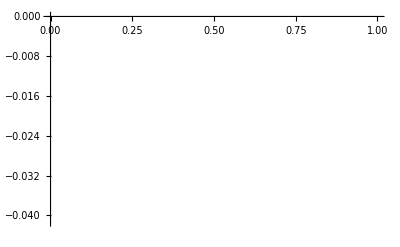

```mathematica
ListLinePlot[{fitData[[1,1]]}]
```

```mathematica
fitData[[3,1]]
```

-0.284444

```mathematica
Table[{dtau[[ii]],fitData[[1,ii]]},{ii,1,3}]
```

(0.2 | -0.020651612227
0.4 | -0.0206516
0.8 | -0.0206516)

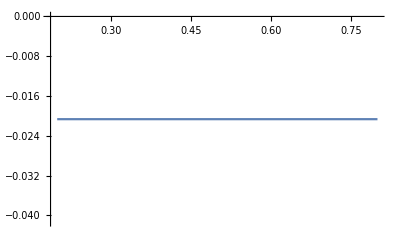

```mathematica
ListLinePlot[{Table[{dtau[[ii]],fitData[[1,ii]]},{ii,1,3}]}]
```

```mathematica
times={1.1,2.3,2.9};(*list of x values*)states={{2.2,4.3,5.5},{2.1,4.6,5.9},{2,4.8,6.2}};(*lists of y values*)td=TemporalData[fitData,{dtau}];
```

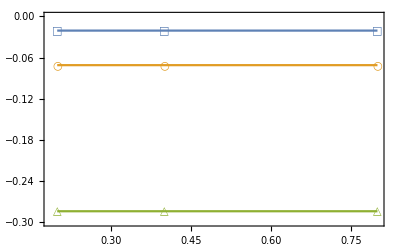

```mathematica
tauScaleCheck=Show[{ListLinePlot[td,PlotRange->{-.3,0},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3]},PlotStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3]}]},Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\delta\\tau",Magnification->1.2],MaTeX["\\Delta E_{QQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3\\text{ (LO)}",Magnification->1.2]]
```

#### QCD NLO - HWF

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={380,380,380};
NWalkers=200;
Nf4α1LoopBig={0.229421,0.4,0.8};
dtau={0.2,0.4,0.8};
aList={1,1,1};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
fitData=Table[Table[Around[Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau[[xx]]]<>"_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[yy]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,3]],Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau[[xx]]]<>"_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[yy]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,4]]],{xx,1,Length[aList]}],{yy,1,Length[aList]}]/."nan":>0
```

(-0.06070.0007 | -0.060510.00026 | -0.06200.0005
-0.23030.0034 | -0.22820.0007 | -0.2310.006
-1.1300.007 | -1.11. | -1.6.)

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][ii]],{ii,1,3}],{MaTeX["a=.2",Magnification->0.8],MaTeX["a=.4",Magnification->0.8],MaTeX["a=.8",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][ii]],{ii,3}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

```mathematica
td=TemporalData[fitData,{dtau}];
```

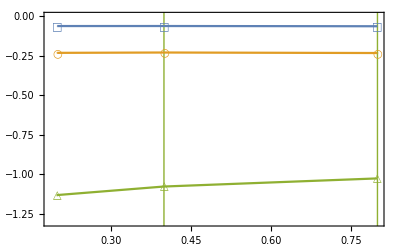

```mathematica
tauScaleCheck=Show[{ListLinePlot[td,PlotRange->{-1.3,0
},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3]},PlotStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3]}]},Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\delta\\tau",Magnification->1.2],MaTeX["\\Delta E_{QQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3\\text{ (NLO)}",Magnification->1.2]]
```

#### QCD mNLO - HWF

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={380,380,380};
NWalkers=200;
Nf4α1LoopBig={0.229421,0.4,0.8};
dtau={0.2,0.4,0.8};
aList={1,1,1};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
fitData=Table[Table[Around[Import[datadir<>"Hammys_mNLO_dtau"<>ToString[dtau[[xx]]]<>"_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[yy]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,3]],Import[datadir<>"Hammys_mNLO_dtau"<>ToString[dtau[[xx]]]<>"_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[yy]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,4]]],{xx,1,Length[aList]}],{yy,1,Length[aList]}]/."nan":>0
```

(-0.07560.0009 | 0.03.3 | -0.07130.0008
0.10. | 0.7. | 0.4.
-1.5. | -1.15. | -2.16.)

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][ii]],{ii,1,3}],{MaTeX["a=.2",Magnification->0.8],MaTeX["a=.4",Magnification->0.8],MaTeX["a=.8",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][ii]],{ii,3}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

```mathematica
td=TemporalData[fitData,{dtau}];
```

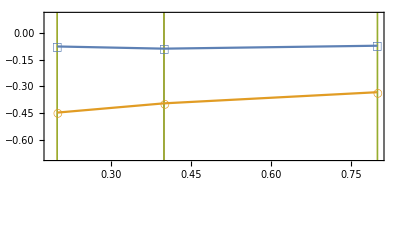

```mathematica
tauScaleCheck=Show[{ListLinePlot[td,PlotRange->{-.7,0.1},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3]},PlotStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3]}]},Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\delta\\tau",Magnification->1.2],MaTeX["\\Delta E_{QQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3\\text{ (mNLO)}",Magnification->1.2]]
```

#### QCD NNLO - HWF

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={393,393,393};
NWalkers=200;
Nf4α1LoopBig={0.225626,0.4,0.8};
dtau={0.2,0.4,0.8};
aList={1,1,1};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
fitData=Table[Table[Around[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau[[xx]]]<>"_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[yy]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,3]],Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau[[xx]]]<>"_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[yy]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,4]]],{xx,1,Length[aList]}],{yy,1,Length[aList]}]/."nan":>0
```

(-0.09880.0007 | -0.10380.0006 | -0.10570.0004
-0.5380.015 | -0.5630.004 | -0.61.9
-4.16. | -4.12. | 0)

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][ii]],{ii,1,3}],{MaTeX["a=.2",Magnification->0.8],MaTeX["a=.4",Magnification->0.8],MaTeX["a=.8",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][ii]],{ii,3}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

```mathematica
td=TemporalData[fitData,{dtau}];
```

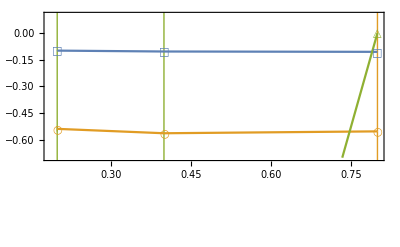

```mathematica
tauScaleCheck=Show[{ListLinePlot[td,PlotRange->{-.7,0.1},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3]},PlotStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3]}]},Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\delta\\tau",Magnification->1.2],MaTeX["\\Delta E_{QQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3\\text{ (NNLO)}",Magnification->1.2]]
```

### baryons

#### QCD LO - HWF

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={430,430,430,430,430,430,430};
NWalkers=200;
Nf4α1LoopBig={0.21556(*,0.21556,0.21556,0.21556,0.21556,0.21556,0.21556*)};
dtau={0.2,0.4,0.8,1.6,3.2,6.4,12.8};
aList={1(*,1,1,1,1,1,1*)};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
fitData=Table[Table[Around[Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau[[xx]]]<>"_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[yy]]]<>"_spoila"<>ToString[aList[[yy]]]<>"_spoilfhwf.csv"][[2,3]],Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau[[xx]]]<>"_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[yy]]]<>"_spoila"<>ToString[aList[[yy]]]<>"_spoilfhwf.csv"][[2,4]]],{xx,1,Length[dtau]}],{yy,1,Length[aList]}]/."nan":>0
```

(-0.0221360.000014 | -0.0221460.000013 | -0.0221357 | -0.0221098 | -0.0221537 | -0.0221458 | -0.0219954)

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][ii]],{ii,1,7}],{MaTeX["\\alpha=.2",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][ii]],{ii,7}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

```mathematica
fitData[[3,1]]
```

(-0.0221360.000014 | -0.0221460.000013 | -0.0221357 | -0.0221098 | -0.0221537 | -0.0221458 | -0.0219954)⟦3,1⟧

```mathematica
Table[{dtau[[ii]],fitData[[1,ii]]},{ii,1,Length[dtau]}]
```

(0.2 | -0.0221360.000014
0.4 | -0.0221460.000013
0.8 | -0.0221357
1.6 | -0.0221098
3.2 | -0.0221537
6.4 | -0.0221458
12.8 | -0.0219954)

```mathematica
times={1.1,2.3,2.9};(*list of x values*)states={{2.2,4.3,5.5},{2.1,4.6,5.9},{2,4.8,6.2}};(*lists of y values*)td=TemporalData[fitData,{dtau}];
```

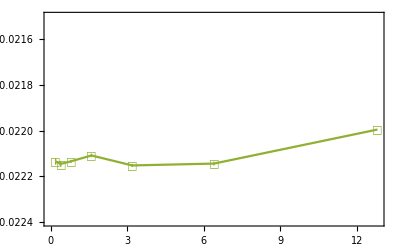

```mathematica
tauScaleCheck=Show[{ListLinePlot[td,PlotRange->{-.0224,-0.0215},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3]},PlotStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3]}]},Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\delta\\tau",Magnification->1.2],MaTeX["\\Delta E_{QQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3\\text{ (LO)}",Magnification->1.2]]
```

#### QCD NLO - HWF

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={380,380,380};
NWalkers=200;
Nf4α1LoopBig={0.229421,0.4,0.8};
dtau={0.2,0.4,0.8};
aList={1,1,1};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
fitData=Table[Table[Around[Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau[[xx]]]<>"_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[yy]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,3]],Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau[[xx]]]<>"_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[yy]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,4]]],{xx,1,Length[aList]}],{yy,1,Length[aList]}]/."nan":>0
```

(-0.06930.0005 | -0.07200.0007 | -0.073040.00027
-0.27980.0013 | -0.28040.0007 | -0.27940.0008
-1.4440.006 | -1.42.2 | -1.33.0)

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][ii]],{ii,1,3}],{MaTeX["a=.2",Magnification->0.8],MaTeX["a=.4",Magnification->0.8],MaTeX["a=.8",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][ii]],{ii,3}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

```mathematica
td=TemporalData[fitData,{dtau}];
```

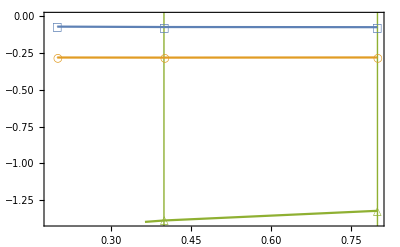

```mathematica
tauScaleCheck=Show[{ListLinePlot[td,PlotRange->{-1.4,0},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3]},PlotStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3]}]},Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\delta\\tau",Magnification->1.2],MaTeX["\\Delta E_{QQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3\\text{ (NLO)}",Magnification->1.2]]
```

#### QCD mNLO - HWF

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={380,380,380};
NWalkers=200;
Nf4α1LoopBig={0.229421,0.4,0.8};
dtau={0.2,0.4,0.8};
aList={1,1,1};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
fitData=Table[Table[Around[Import[datadir<>"Hammys_mNLO_dtau"<>ToString[dtau[[xx]]]<>"_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[yy]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,3]],Import[datadir<>"Hammys_mNLO_dtau"<>ToString[dtau[[xx]]]<>"_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[yy]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,4]]],{xx,1,Length[aList]}],{yy,1,Length[aList]}]/."nan":>0
```

(-0.07780.0006 | -0.08130.0006 | 0.6.
0.4. | -0.30.9 | 0.21.
-1.42.2 | -2.4. | 0)

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][ii]],{ii,1,3}],{MaTeX["a=.2",Magnification->0.8],MaTeX["a=.4",Magnification->0.8],MaTeX["a=.8",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][ii]],{ii,3}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

```mathematica
td=TemporalData[fitData,{dtau}];
```

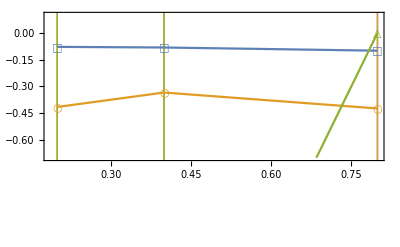

```mathematica
tauScaleCheck=Show[{ListLinePlot[td,PlotRange->{-.7,0.1},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3]},PlotStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3]}]},Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\delta\\tau",Magnification->1.2],MaTeX["\\Delta E_{QQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3\\text{ (mNLO)}",Magnification->1.2]]
```

#### QCD NNLO - HWF

```mathematica
Nf4α1LoopMid
Nf4α1LoopStepTab={393,393,393};
NWalkers=200;
Nf4α1LoopBig={0.225626,0.4,0.8};
dtau={0.2,0.4,0.8};
aList={1,1,1};
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
fitData=Table[Table[Around[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau[[xx]]]<>"_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[yy]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,3]],Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau[[xx]]]<>"_Nstep"<>ToString[Nf4α1LoopStepTab[[xx]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3"<>"_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[yy]]]<>"_spoila"<>ToString[aList[[xx]]]<>"_spoilfhwf.csv"][[2,4]]],{xx,1,Length[aList]}],{yy,1,Length[aList]}]/."nan":>0
```

(-0.12050.0010 | -0.12850.0007 | -0.13000.0005
-0.7290.004 | -0.6940.004 | -0.71.7
-6.11. | 0 | 0)

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][ii]],{ii,1,3}],{MaTeX["a=.2",Magnification->0.8],MaTeX["a=.4",Magnification->0.8],MaTeX["a=.8",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][ii]],{ii,3}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

```mathematica
td=TemporalData[fitData,{dtau}];
```

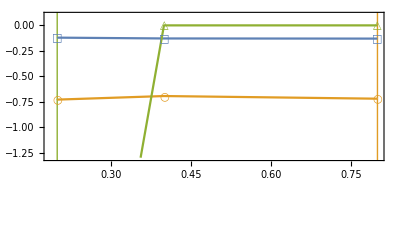

```mathematica
tauScaleCheck=Show[{ListLinePlot[td,PlotRange->{-1.3,0.1},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3]},PlotStyle->{ColorData[97][1],ColorData[97][2],ColorData[97][3]}]},Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\delta\\tau",Magnification->1.2],MaTeX["\\Delta E_{QQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["N=3\\text{ (NNLO)}",Magnification->1.2]]
```